# Circulant Graph

### Author

Eric W. Weisstein
January 30, 2008

This notebook downloaded from http://mathworld.wolfram.com/notebooks/GraphTheory/CirculantGraph.nb.

For more information, see Eric's MathWorld entry http://mathworld.wolfram.com/CirculantGraph.html.

For a list of Eric's math packages that may be needed to evaluate this notebook, see Mathematica Information Center's MathSource item 4775.  A list of Eric's utility packages that may be needed to evaluate this notebook may be downloaded from MathSource item 5087.

©2008 Wolfram Research, Inc. except for portions noted otherwise

### Initialization

```mathematica
<<MathWorld`Graphs`
```

NautyTools Beta 0.2.0 by Mike Pilat, modified by Eric Weisstein

Based on NAUTY 2.2 by Brendan McKay

### Typesetting

```mathematica
MakeBoxes[Circulant[n_,l_],TraditionalForm]:=RowBox[{SubscriptBox["Ci",MakeBoxes[n,TraditionalForm]],"(",RowBox[Riffle[l,","]],")"}]
```

### Usage

```mathematica
?CirculantGraph
```

CirculantGraph[n,l] constructs a circulant graph on n vertices, meaning the i^th vertex is adjacent to the (i+j)^th and (i-j)^th vertices, for each j in list l. 
CirculantGraph[n,l] returns the graph with n vertices in which each i is adjacent to (i+l) and (i-l), where l must be an integer.

## Random

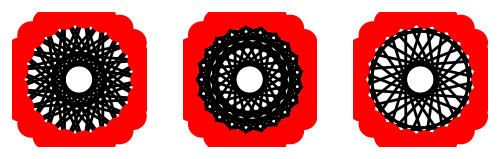

```mathematica
Show[GraphicsArray[Table[ShowGraph[CirculantGraph[21,RandomKSubset[Range[10],3]]],{3}]],ImageSize->500]
```

## Table

```mathematica
l=CirculantGraphQ[GraphData[#,"Automorphisms"]]&/@(g=Select[GraphData[],Head[GraphData[#,"Automorphisms"]]=!=Missing&]);//Timing
```

{1.70761,Null}

```mathematica
circ=Union[First[Flatten[{#}]]&/@GraphData["Circulant"]]
```

{Antiprism,Circulant,CocktailParty,Complete,CompleteBipartite,Crown,Cycle,Empty,Haar,LadderRung,Lattice,MoebiusLadder,OctahedralGraph,Paley,Path,PentatopeGraph,Prism,Sextic,SixteenCellGraph,SquareGraph,TetrahedralGraph,TorusGrid,TriangleGraph,UtilityGraph}

```mathematica
{#,Complement[GraphData[#],GraphData[{#,"Circulant"}]]}&/@Select[circ,ListQ[GraphData[#]]&]//Column
```

{Antiprism,{}}
{Circulant,{}}
{CocktailParty,{}}
{Complete,{SingletonGraph}}
{CompleteBipartite,{Claw,{CompleteBipartite,{2,3}},{CompleteBipartite,{2,4}},{CompleteBipartite,{2,5}},{CompleteBipartite,{2,6}},{CompleteBipartite,{2,7}},{CompleteBipartite,{2,8}},{CompleteBipartite,{2,9}},{CompleteBipartite,{2,10}},{CompleteBipartite,{3,4}},{CompleteBipartite,{3,5}},{CompleteBipartite,{3,6}},{CompleteBipartite,{3,7}},{CompleteBipartite,{3,8}},{CompleteBipartite,{3,9}},{CompleteBipartite,{3,10}},{CompleteBipartite,{4,5}},{CompleteBipartite,{4,6}},{CompleteBipartite,{4,7}},{CompleteBipartite,{4,8}},{CompleteBipartite,{4,9}},{CompleteBipartite,{4,10}},{CompleteBipartite,{5,6}},{CompleteBipartite,{5,7}},{CompleteBipartite,{5,8}},{CompleteBipartite,{5,9}},{CompleteBipartite,{5,10}},{CompleteBipartite,{6,7}},{CompleteBipartite,{6,8}},{CompleteBipartite,{6,9}},{CompleteBipartite,{6,10}},{CompleteBipartite,{7,8}},{CompleteBipartite,{7,9}},{CompleteBipartite,{7,10}},{CompleteBipartite,{8,9}},{CompleteBipartite,{8,10}},{CompleteBipartite,{9,10}},{Path,3},{Star,5},{Star,6},{Star,7},{Star,8},{Star,9},{Star,10},{Star,11},{Star,12},{Star,13},{Star,14},{Star,15},{Star,16},{Star,17},{Star,18},{Star,19},{Star,20}}}
{Crown,{CubicalGraph,{Crown,6},{Crown,8},{Crown,10},{Crown,12},{Crown,14},{Crown,16},{Crown,18},{Crown,20}}}
{Cycle,{}}
{Empty,{SingletonGraph,{Empty,21},{Empty,22},{Empty,23},{Empty,24},{Empty,25},{Empty,26},{Empty,27},{Empty,28},{Empty,29},{Empty,30}}}
{Haar,{CubicalGraph,Foster026A,FranklinGraph,HeawoodGraph,MoebiusKantorGraph,{Cage,{4,6}},{CrossedPrism,8},{CrossedPrism,10},{CrossedPrism,12},{CrossedPrism,14},{CrossedPrism,16},{CrossedPrism,18},{CrossedPrism,20},{Crown,6},{Crown,8},{Crown,10},{Crown,12},{Crown,14},{Crown,16},{Crown,18},{Crown,20},{CubicTransitive,20},{CubicTransitive,25},{CubicTransitive,32},{CubicTransitive,35},{CubicTransitive,36},{CubicTransitive,38},{CubicTransitive,47},{CubicTransitive,51},{CubicTransitive,52},{CubicTransitive,58},{CubicTransitive,59},{CubicTransitive,60},{CubicTransitive,62},{CubicTransitive,67},{CubicTransitive,68},{GeneralizedPetersen,{16,7}},{Haar,34},{Haar,36},{Haar,130},{Haar,136},{Haar,138},{Haar,143},{Haar,151},{Haar,155},{Haar,175},{Haar,187},{Haar,260},{Haar,279},{Haar,301},{Haar,303},{Haar,514},{Haar,522},{Haar,523},{Haar,525},{Haar,527},{Haar,528},{Haar,531},{Haar,533},{Haar,535},{Haar,539},{Haar,547},{Haar,551},{Haar,554},{Haar,555},{Haar,558},{Haar,559},{Haar,563},{Haar,565},{Haar,567},{Haar,571},{Haar,575},{Haar,591},{Haar,599},{Haar,607},{Haar,631},{Haar,682},{Haar,683},{Haar,687},{Haar,703},{Incidence,{11,5,2}},{Incidence,{15,7,3}},{LadderRung,4},{LadderRung,5},{LadderRung,6},{LadderRung,7},{LadderRung,8},{LadderRung,9},{LadderRung,10},{LadderRung,11},{LadderRung,12},{LadderRung,13},{LadderRung,14},{LadderRung,15},{LadderRung,16},{LadderRung,17},{LadderRung,18},{LadderRung,19},{LadderRung,20},{Prism,6},{Prism,8},{Prism,10},{Prism,12},{Prism,14},{Prism,16},{Prism,18},{Prism,20},{QuarticTransitive,23},{QuarticTransitive,31},{QuarticTransitive,40},{QuarticTransitive,48},{QuarticTransitive,57},{QuarticTransitive,67},{Quintic,{16,1}}}}
{LadderRung,{{LadderRung,4},{LadderRung,5},{LadderRung,6},{LadderRung,7},{LadderRung,8},{LadderRung,9},{LadderRung,10},{LadderRung,11},{LadderRung,12},{LadderRung,13},{LadderRung,14},{LadderRung,15},{LadderRung,16},{LadderRung,17},{LadderRung,18},{LadderRung,19},{LadderRung,20}}}
{Lattice,{{GeneralizedQuadrangle,{2,1}},{Lattice,{2,4}},{Lattice,{2,6}},{Lattice,{2,8}},{Lattice,{2,10}},{Lattice,{3,6}},{Lattice,{3,9}},{Lattice,{4,4}},{Lattice,{4,6}},{Lattice,{4,8}},{Lattice,{4,10}},{Lattice,{5,5}},{Lattice,{5,10}},{Lattice,{6,6}},{Lattice,{6,8}},{Lattice,{6,9}},{Lattice,{6,10}},{Lattice,{7,7}},{Lattice,{8,8}},{Lattice,{8,10}},{Lattice,{9,9}},{Lattice,{10,10}}}}
{MoebiusLadder,{}}
{Paley,{{GeneralizedQuadrangle,{2,1}},{Paley,25},{Paley,49},{Paley,81},{Paley,121},{Paley,125},{Paley,169}}}
{Path,{SingletonGraph,{Path,3},{Path,4},{Path,5},{Path,6},{Path,7},{Path,8},{Path,9},{Path,10},{Path,11},{Path,12},{Path,13},{Path,14},{Path,15},{Path,16},{Path,17},{Path,18},{Path,19},{Path,20}}}
{Prism,{CubicalGraph,{Grid,{2,2,3}},{Grid,{2,2,4}},{Grid,{2,2,5}},{Prism,6},{Prism,8},{Prism,10},{Prism,12},{Prism,14},{Prism,16},{Prism,18},{Prism,20},{Prism,{3,3}},{Prism,{3,4}},{Prism,{3,5}},{Prism,{5,3}},{Prism,{5,4}},{Prism,{5,5}},{Prism,{6,3}},{Prism,{6,4}},{Prism,{6,5}},{Prism,{7,3}},{Prism,{7,4}},{Prism,{7,5}},{Prism,{8,3}},{Prism,{8,4}},{Prism,{8,5}}}}
{Sextic,{HoffmanSingletonMinusStar,KummerGraph,PerkelGraph,ReyeGraph,ShrikhandeGraph,{Cage,{6,5}},{Cage,{6,6}},{Cone,{6,4}},{GeneralizedHexagon,{3,1}},{GeneralizedQuadrangle,{2,2}},{Haar,175},{Haar,187},{Haar,303},{Haar,559},{Haar,567},{Haar,571},{Haar,591},{Haar,599},{Haar,683},{Hypercube,6},{Lattice,{2,6}},{Lattice,{4,4}},{Odd,6},{Sextic,{9,1}},{Sextic,{9,2}},{Sextic,{10,1}},{Sextic,{10,2}},{Sextic,{10,3}},{Sextic,{10,4}},{Sextic,{10,5}},{Sextic,{10,6}},{Sextic,{10,9}},{Sextic,{10,10}},{Sextic,{10,11}},{Sextic,{10,12}},{Sextic,{10,13}},{Sextic,{10,14}},{Sextic,{10,15}},{Sextic,{10,16}},{Sextic,{10,17}},{Sextic,{10,20}},{Sextic,{10,21}},{Sextic,{11,162}},{Sextic,{11,163}},{Sextic,{11,164}},{Sextic,{11,165}},{Sextic,{11,166}},{Sextic,{11,167}},{Sextic,{11,168}},{Sextic,{11,169}},{Sextic,{11,170}},{Sextic,{11,171}},{Sextic,{11,172}},{Sextic,{11,173}},{Sextic,{11,174}},{Sextic,{11,175}},{Sextic,{11,176}},{Sextic,{11,177}},{Sextic,{11,178}},{Sextic,{11,179}},{Sextic,{11,180}},{Sextic,{11,181}},{Sextic,{11,182}},{Sextic,{11,183}},{Sextic,{11,184}},{Sextic,{11,185}},{Sextic,{11,186}},{Sextic,{11,187}},{Sextic,{11,188}},{Sextic,{11,189}},{Sextic,{11,190}},{Sextic,{11,191}},{Sextic,{11,192}},{Sextic,{11,193}},{Sextic,{11,194}},{Sextic,{11,195}},{Sextic,{11,196}},{Sextic,{11,197}},{Sextic,{11,198}},{Sextic,{11,199}},{Sextic,{11,200}},{Sextic,{11,201}},{Sextic,{11,202}},{Sextic,{11,203}},{Sextic,{11,204}},{Sextic,{11,205}},{Sextic,{11,206}},{Sextic,{11,207}},{Sextic,{11,208}},{Sextic,{11,209}},{Sextic,{11,210}},{Sextic,{11,211}},{Sextic,{11,212}},{Sextic,{11,213}},{Sextic,{11,214}},{Sextic,{11,215}},{Sextic,{11,216}},{Sextic,{11,217}},{Sextic,{11,218}},{Sextic,{11,219}},{Sextic,{11,220}},{Sextic,{11,221}},{Sextic,{11,222}},{Sextic,{11,223}},{Sextic,{11,224}},{Sextic,{11,225}},{Sextic,{11,226}},{Sextic,{11,227}},{Sextic,{11,228}},{Sextic,{11,229}},{Sextic,{11,230}},{Sextic,{11,231}},{Sextic,{11,232}},{Sextic,{11,233}},{Sextic,{11,234}},{Sextic,{11,235}},{Sextic,{11,236}},{Sextic,{11,237}},{Sextic,{11,238}},{Sextic,{11,239}},{Sextic,{11,240}},{Sextic,{11,241}},{Sextic,{11,242}},{Sextic,{11,243}},{Sextic,{11,244}},{Sextic,{11,245}},{Sextic,{11,246}},{Sextic,{11,247}},{Sextic,{11,248}},{Sextic,{11,249}},{Sextic,{11,250}},{Sextic,{11,251}},{Sextic,{11,252}},{Sextic,{11,253}},{Sextic,{11,254}},{Sextic,{11,255}},{Sextic,{11,256}},{Sextic,{11,257}},{Sextic,{11,258}},{Sextic,{11,259}},{Sextic,{11,260}},{Sextic,{11,261}},{Sextic,{11,262}},{Sextic,{11,263}},{Sextic,{11,264}},{Sextic,{11,265}},{Sextic,{12,1}},{Sextic,{12,2}},{Sextic,{12,3}},{Sextic,{14,1}},{Sextic,{16,2}},{Triangular,5}}}
{TorusGrid,{{TorusGrid,{3,4}},{TorusGrid,{4,5}},{TorusGrid,{4,6}},{TorusGrid,{4,7}},{TorusGrid,{4,8}}}}

```mathematica
{#,GraphData[{"Circulant",#}]}&/@{"CompleteBipartite","Crown","Haar","Lattice","TorusGrid"}//Column
```

{CompleteBipartite,{{CompleteBipartite,{4,4}},{CompleteBipartite,{5,5}},{CompleteBipartite,{6,6}},{CompleteBipartite,{7,7}},{CompleteBipartite,{8,8}},{CompleteBipartite,{9,9}},{CompleteBipartite,{10,10}},{CompleteBipartite,{11,11}},{CompleteBipartite,{12,12}},{CompleteBipartite,{13,13}},{CompleteBipartite,{14,14}},{CompleteBipartite,{15,15}},{CompleteBipartite,{16,16}},{CompleteBipartite,{17,17}},{CompleteBipartite,{18,18}},{CompleteBipartite,{19,19}},{CompleteBipartite,{20,20}},{Path,2},SquareGraph,UtilityGraph}}
{Crown,{{Crown,5},{Crown,7},{Crown,9},{Crown,11},{Crown,13},{Crown,15},{Crown,17},{Crown,19},{Cycle,6}}}
{Haar,{{Circulant,{12,{1,3}}},{Circulant,{12,{1,5}}},{Circulant,{12,{2,6}}},{Circulant,{14,{1,3}}},{Circulant,{14,{1,3,7}}},{Circulant,{16,{1,3}}},{Circulant,{16,{1,7}}},{Circulant,{16,{2,6}}},{Circulant,{18,{1,3}}},{Circulant,{18,{1,5}}},{Circulant,{18,{3,9}}},{CompleteBipartite,{4,4}},{CompleteBipartite,{5,5}},{CompleteBipartite,{6,6}},{CompleteBipartite,{7,7}},{CompleteBipartite,{8,8}},{CompleteBipartite,{9,9}},{CompleteBipartite,{10,10}},{CompleteBipartite,{11,11}},{CompleteBipartite,{12,12}},{CompleteBipartite,{13,13}},{CompleteBipartite,{14,14}},{CompleteBipartite,{15,15}},{CompleteBipartite,{16,16}},{Crown,5},{Crown,7},{Crown,9},{Crown,11},{Crown,13},{Crown,15},{Crown,17},{Crown,19},{Cycle,6},{Cycle,8},{Cycle,10},{Cycle,12},{Cycle,14},{Cycle,16},{Cycle,18},{Cycle,20},{Haar,159},{Haar,271},{Haar,287},{Haar,295},{Haar,319},{Haar,365},{Haar,367},{Haar,519},{Haar,534},{Haar,543},{Haar,561},{Haar,606},{Haar,627},{Haar,639},{Haar,759},{LadderRung,2},{LadderRung,3},{MoebiusLadder,5},{MoebiusLadder,7},{MoebiusLadder,9},{MoebiusLadder,11},{MoebiusLadder,13},{MoebiusLadder,15},{MoebiusLadder,17},{MoebiusLadder,19},{Path,2},SquareGraph,UtilityGraph}}
{Lattice,{{Circulant,{10,{2,4,5}}},{Circulant,{12,{3,4,6}}},{Circulant,{14,{2,4,6,7}}},{Lattice,{2,9}},{Lattice,{3,7}},{Lattice,{3,8}},{Lattice,{3,10}},{Lattice,{4,5}},{Lattice,{4,7}},{Lattice,{4,9}},{Lattice,{5,6}},{Lattice,{5,7}},{Lattice,{5,8}},{Lattice,{5,9}},{Lattice,{6,7}},{Lattice,{7,8}},{Lattice,{7,9}},{Lattice,{7,10}},{Lattice,{8,9}},{Lattice,{9,10}},{Prism,3},SquareGraph}}
{TorusGrid,{{Complete,6},SixteenCellGraph,{TorusGrid,{5,5}},{TorusGrid,{6,6}},{TorusGrid,{8,8}},{TorusGrid,{9,9}},{TorusGrid,{10,10}}}}

```mathematica
{#[[2]],Circulant@@#[[1]]}&/@Take[Sort[{"Circulant"/.GraphData[#,"NotationRules"],GraphData[#,"Name"]}&/@DeleteCases[GraphData[{"Circulant","Connected"}],{"Circulant",_}]],30]//TableForm//TraditionalForm
```

2-path graph | Ci_2(1)
triangle graph | Ci_3(1)
square graph | Ci_4(1)
tetrahedral graph | Ci_4(1,2)
5-cycle graph | Ci_5(1)
pentatope graph | Ci_5(1,2)
6-cycle graph | Ci_6(1)
octahedral graph | Ci_6(1,2)
utility graph | Ci_6(1,3)
3-prism graph | Ci_6(2,3)
6-complete graph | Ci_6(1,2,3)
7-cycle graph | Ci_7(1)
7-complete graph | Ci_7(1,2,3)
8-cycle graph | Ci_8(1)
4-antiprism graph | Ci_8(1,2)
(4,4)-complete bipartite graph | Ci_8(1,3)
4-Möbius ladder graph | Ci_8(1,4)
16-cell graph | Ci_8(1,2,3)
8-complete graph | Ci_8(1,2,3,4)
9-cycle graph | Ci_9(1)
9-complete graph | Ci_9(1,2,3,4)
10-cycle graph | Ci_10(1)
5-antiprism graph | Ci_10(1,2)
5-crown graph | Ci_10(1,3)
5-Möbius ladder graph | Ci_10(1,5)
5-prism graph | Ci_10(2,5)
(5,5)-complete bipartite graph | Ci_10(1,3,5)
5-cocktail party graph | Ci_10(1,2,3,4)
(5,5)-torus grid graph | Ci_10(1,2,3,5)
10-complete graph | Ci_10(1,2,3,4,5)

## In terms of Complete Bipartite Graphs

```mathematica
g=RecognizeGraph/@Table[CompleteGraph[n,n],{n,8}]
```

RecognizeGraph::type1: Graph is of type "Path"[2]

RecognizeGraph::type1: Graph is of type "Cycle"[4]

RecognizeGraph::type2: Graph is of type "CirculantGraph"[6,{1, 3}]

RecognizeGraph::type2: Graph is of type "CirculantGraph"[8,{1, 3}]

RecognizeGraph::type2: Graph is of type "CirculantGraph"[10,{1, 3, 5}]

RecognizeGraph::type2: Graph is of type "CirculantGraph"[12,{1, 3, 5}]

RecognizeGraph::type2: Graph is of type "CirculantGraph"[14,{1, 3, 5, 7}]

RecognizeGraph::type2: Graph is of type "CirculantGraph"[16,{1, 3, 5, 7}]

{⁃Graph:<1, 2, Undirected>⁃,⁃Graph:<4, 4, Undirected>⁃,⁃Graph:<9, 6, Undirected>⁃,⁃Graph:<16, 8, Undirected>⁃,⁃Graph:<25, 10, Undirected>⁃,⁃Graph:<36, 12, Undirected>⁃,⁃Graph:<49, 14, Undirected>⁃,⁃Graph:<64, 16, Undirected>⁃}

```mathematica
ShowGraphArray[Rest[g],
VertexStyle->Disk[.08],
VertexColor->Red,
AspectRatio->Automatic]
```

⁃GraphicsArray⁃

```mathematica
PlanarQ/@g
```

{True,True,False,False,False,False,False,False}

## Enumeration

```mathematica
Timing[Length/@(circ=Table[Select[Graphs[n],CirculantGraphQ],{n,8}])]
```

{12473. Second,{0,1,1,3,2,7,3,11}}

### Input

```mathematica
circ//InputForm
```

{{}, {Graph[{{{1, 2}}}, {{{-1., 0}}, {{1., 0}}}]}, 
 {Graph[{{{1, 2}}, {{1, 3}}, {{2, 3}}}, {{{-0.49999999999999983, 0.8660254037844387}}, 
    {{-0.5000000000000004, -0.8660254037844384}}, {{1., 0}}}]}, 
 {Graph[{{{1, 3}}, {{2, 4}}}, {{{0, 1.}}, {{-1., 0}}, {{0, -1.}}, {{1., 0}}}], 
  Graph[{{{1, 3}}, {{1, 4}}, {{2, 3}}, {{2, 4}}}, {{{0, 1.}}, {{-1., 0}}, {{0, -1.}}, 
    {{1., 0}}}], Graph[{{{1, 2}}, {{1, 3}}, {{1, 4}}, {{2, 3}}, {{2, 4}}, {{3, 4}}}, 
   {{{0, 1.}}, {{-1., 0}}, {{0, -1.}}, {{1., 0}}}]}, 
 {Graph[{{{1, 3}}, {{1, 4}}, {{2, 4}}, {{2, 5}}, {{3, 5}}}, 
   {{{0.3090169943749475, 0.9510565162951535}}, 
    {{-0.8090169943749473, 0.5877852522924732}}, 
    {{-0.8090169943749476, -0.587785252292473}}, 
    {{0.30901699437494723, -0.9510565162951536}}, {{1., 0}}}], 
  Graph[{{{1, 2}}, {{1, 3}}, {{1, 4}}, {{1, 5}}, {{2, 3}}, {{2, 4}}, {{2, 5}}, 
    {{3, 4}}, {{3, 5}}, {{4, 5}}}, {{{0.3090169943749475, 0.9510565162951535}}, 
    {{-0.8090169943749473, 0.5877852522924732}}, 
    {{-0.8090169943749476, -0.587785252292473}}, 
    {{0.30901699437494723, -0.9510565162951536}}, {{1., 0}}}]}, 
 {Graph[{{{1, 4}}, {{2, 5}}, {{3, 6}}}, {{{0.5000000000000001, 0.8660254037844386}}, 
    {{-0.49999999999999983, 0.8660254037844387}}, {{-1., 0}}, 
    {{-0.5000000000000004, -0.8660254037844384}}, 
    {{0.49999999999999933, -0.866025403784439}}, {{1., 0}}}], 
  Graph[{{{1, 4}}, {{1, 5}}, {{2, 4}}, {{2, 6}}, {{3, 5}}, {{3, 6}}}, 
   {{{0.5000000000000001, 0.8660254037844386}}, 
    {{-0.49999999999999983, 0.8660254037844387}}, {{-1., 0}}, 
    {{-0.5000000000000004, -0.8660254037844384}}, 
    {{0.49999999999999933, -0.866025403784439}}, {{1., 0}}}], 
  Graph[{{{1, 4}}, {{1, 5}}, {{1, 6}}, {{2, 4}}, {{2, 5}}, {{2, 6}}, {{3, 4}}, 
    {{3, 5}}, {{3, 6}}}, {{{0.5000000000000001, 0.8660254037844386}}, 
    {{-0.49999999999999983, 0.8660254037844387}}, {{-1., 0}}, 
    {{-0.5000000000000004, -0.8660254037844384}}, 
    {{0.49999999999999933, -0.866025403784439}}, {{1., 0}}}], 
  Graph[{{{1, 3}}, {{1, 5}}, {{2, 4}}, {{2, 6}}, {{3, 5}}, {{4, 6}}}, 
   {{{0.5000000000000001, 0.8660254037844386}}, 
    {{-0.49999999999999983, 0.8660254037844387}}, {{-1., 0}}, 
    {{-0.5000000000000004, -0.8660254037844384}}, 
    {{0.49999999999999933, -0.866025403784439}}, {{1., 0}}}], 
  Graph[{{{1, 3}}, {{1, 4}}, {{1, 5}}, {{2, 4}}, {{2, 5}}, {{2, 6}}, {{3, 5}}, 
    {{3, 6}}, {{4, 6}}}, {{{0.5000000000000001, 0.8660254037844386}}, 
    {{-0.49999999999999983, 0.8660254037844387}}, {{-1., 0}}, 
    {{-0.5000000000000004, -0.8660254037844384}}, 
    {{0.49999999999999933, -0.866025403784439}}, {{1., 0}}}], 
  Graph[{{{1, 3}}, {{1, 4}}, {{1, 5}}, {{1, 6}}, {{2, 3}}, {{2, 4}}, {{2, 5}}, 
    {{2, 6}}, {{3, 5}}, {{3, 6}}, {{4, 5}}, {{4, 6}}}, 
   {{{0.5000000000000001, 0.8660254037844386}}, 
    {{-0.49999999999999983, 0.8660254037844387}}, {{-1., 0}}, 
    {{-0.5000000000000004, -0.8660254037844384}}, 
    {{0.49999999999999933, -0.866025403784439}}, {{1., 0}}}], 
  Graph[{{{1, 2}}, {{1, 3}}, {{1, 4}}, {{1, 5}}, {{1, 6}}, {{2, 3}}, {{2, 4}}, 
    {{2, 5}}, {{2, 6}}, {{3, 4}}, {{3, 5}}, {{3, 6}}, {{4, 5}}, {{4, 6}}, {{5, 6}}}, 
   {{{0.5000000000000001, 0.8660254037844386}}, 
    {{-0.49999999999999983, 0.8660254037844387}}, {{-1., 0}}, 
    {{-0.5000000000000004, -0.8660254037844384}}, 
    {{0.49999999999999933, -0.866025403784439}}, {{1., 0}}}]}, 
 {Graph[{{{1, 4}}, {{1, 5}}, {{2, 5}}, {{2, 6}}, {{3, 6}}, {{3, 7}}, {{4, 7}}}, 
   {{{0.6234898018587336, 0.7818314824680298}}, 
    {{-0.22252093395631434, 0.9749279121818236}}, 
    {{-0.900968867902419, 0.43388373911755823}}, 
    {{-0.9009688679024191, -0.433883739117558}}, 
    {{-0.2225209339563146, -0.9749279121818236}}, 
    {{0.6234898018587334, -0.7818314824680299}}, {{1., 0}}}], 
  Graph[{{{1, 3}}, {{1, 4}}, {{1, 5}}, {{1, 6}}, {{2, 4}}, {{2, 5}}, {{2, 6}}, 
    {{2, 7}}, {{3, 5}}, {{3, 6}}, {{3, 7}}, {{4, 6}}, {{4, 7}}, {{5, 7}}}, 
   {{{0.6234898018587336, 0.7818314824680298}}, 
    {{-0.22252093395631434, 0.9749279121818236}}, 
    {{-0.900968867902419, 0.43388373911755823}}, 
    {{-0.9009688679024191, -0.433883739117558}}, 
    {{-0.2225209339563146, -0.9749279121818236}}, 
    {{0.6234898018587334, -0.7818314824680299}}, {{1., 0}}}], 
  Graph[{{{1, 2}}, {{1, 3}}, {{1, 4}}, {{1, 5}}, {{1, 6}}, {{1, 7}}, {{2, 3}}, 
    {{2, 4}}, {{2, 5}}, {{2, 6}}, {{2, 7}}, {{3, 4}}, {{3, 5}}, {{3, 6}}, {{3, 7}}, 
    {{4, 5}}, {{4, 6}}, {{4, 7}}, {{5, 6}}, {{5, 7}}, {{6, 7}}}, 
   {{{0.6234898018587336, 0.7818314824680298}}, 
    {{-0.22252093395631434, 0.9749279121818236}}, 
    {{-0.900968867902419, 0.43388373911755823}}, 
    {{-0.9009688679024191, -0.433883739117558}}, 
    {{-0.2225209339563146, -0.9749279121818236}}, 
    {{0.6234898018587334, -0.7818314824680299}}, {{1., 0}}}]}, 
 {Graph[{{{1, 5}}, {{2, 6}}, {{3, 7}}, {{4, 8}}}, 
   {{{0.7071067811865475, 0.7071067811865476}}, {{0, 1.}}, 
    {{-0.7071067811865475, 0.7071067811865476}}, {{-1., 0}}, 
    {{-0.7071067811865477, -0.7071067811865474}}, {{0, -1.}}, 
    {{0.7071067811865474, -0.7071067811865477}}, {{1., 0}}}], 
  Graph[{{{1, 5}}, {{1, 6}}, {{2, 5}}, {{2, 7}}, {{3, 6}}, {{3, 8}}, {{4, 7}}, 
    {{4, 8}}}, {{{0.7071067811865475, 0.7071067811865476}}, {{0, 1.}}, 
    {{-0.7071067811865475, 0.7071067811865476}}, {{-1., 0}}, 
    {{-0.7071067811865477, -0.7071067811865474}}, {{0, -1.}}, 
    {{0.7071067811865474, -0.7071067811865477}}, {{1., 0}}}], 
  Graph[{{{1, 5}}, {{1, 6}}, {{2, 5}}, {{2, 6}}, {{3, 7}}, {{3, 8}}, {{4, 7}}, 
    {{4, 8}}}, {{{0.7071067811865475, 0.7071067811865476}}, {{0, 1.}}, 
    {{-0.7071067811865475, 0.7071067811865476}}, {{-1., 0}}, 
    {{-0.7071067811865477, -0.7071067811865474}}, {{0, -1.}}, 
    {{0.7071067811865474, -0.7071067811865477}}, {{1., 0}}}], 
  Graph[{{{1, 5}}, {{1, 6}}, {{1, 7}}, {{1, 8}}, {{2, 5}}, {{2, 6}}, {{2, 7}}, 
    {{2, 8}}, {{3, 5}}, {{3, 6}}, {{3, 7}}, {{3, 8}}, {{4, 5}}, {{4, 6}}, {{4, 7}}, 
    {{4, 8}}}, {{{0.7071067811865475, 0.7071067811865476}}, {{0, 1.}}, 
    {{-0.7071067811865475, 0.7071067811865476}}, {{-1., 0}}, 
    {{-0.7071067811865477, -0.7071067811865474}}, {{0, -1.}}, 
    {{0.7071067811865474, -0.7071067811865477}}, {{1., 0}}}], 
  Graph[{{{1, 4}}, {{1, 5}}, {{1, 6}}, {{2, 5}}, {{2, 6}}, {{2, 7}}, {{3, 6}}, 
    {{3, 7}}, {{3, 8}}, {{4, 7}}, {{4, 8}}, {{5, 8}}}, 
   {{{0.7071067811865475, 0.7071067811865476}}, {{0, 1.}}, 
    {{-0.7071067811865475, 0.7071067811865476}}, {{-1., 0}}, 
    {{-0.7071067811865477, -0.7071067811865474}}, {{0, -1.}}, 
    {{0.7071067811865474, -0.7071067811865477}}, {{1., 0}}}], 
  Graph[{{{1, 3}}, {{1, 5}}, {{1, 7}}, {{2, 4}}, {{2, 6}}, {{2, 8}}, {{3, 5}}, 
    {{3, 7}}, {{4, 6}}, {{4, 8}}, {{5, 7}}, {{6, 8}}}, 
   {{{0.7071067811865475, 0.7071067811865476}}, {{0, 1.}}, 
    {{-0.7071067811865475, 0.7071067811865476}}, {{-1., 0}}, 
    {{-0.7071067811865477, -0.7071067811865474}}, {{0, -1.}}, 
    {{0.7071067811865474, -0.7071067811865477}}, {{1., 0}}}], 
  Graph[{{{1, 3}}, {{1, 5}}, {{1, 6}}, {{1, 7}}, {{2, 4}}, {{2, 5}}, {{2, 7}}, 
    {{2, 8}}, {{3, 5}}, {{3, 6}}, {{3, 8}}, {{4, 6}}, {{4, 7}}, {{4, 8}}, {{5, 7}}, 
    {{6, 8}}}, {{{0.7071067811865475, 0.7071067811865476}}, {{0, 1.}}, 
    {{-0.7071067811865475, 0.7071067811865476}}, {{-1., 0}}, 
    {{-0.7071067811865477, -0.7071067811865474}}, {{0, -1.}}, 
    {{0.7071067811865474, -0.7071067811865477}}, {{1., 0}}}], 
  Graph[{{{1, 3}}, {{1, 5}}, {{1, 6}}, {{1, 7}}, {{1, 8}}, {{2, 4}}, {{2, 5}}, 
    {{2, 6}}, {{2, 7}}, {{2, 8}}, {{3, 5}}, {{3, 6}}, {{3, 7}}, {{3, 8}}, {{4, 5}}, 
    {{4, 6}}, {{4, 7}}, {{4, 8}}, {{5, 7}}, {{6, 8}}}, 
   {{{0.7071067811865475, 0.7071067811865476}}, {{0, 1.}}, 
    {{-0.7071067811865475, 0.7071067811865476}}, {{-1., 0}}, 
    {{-0.7071067811865477, -0.7071067811865474}}, {{0, -1.}}, 
    {{0.7071067811865474, -0.7071067811865477}}, {{1., 0}}}], 
  Graph[{{{1, 3}}, {{1, 4}}, {{1, 5}}, {{1, 6}}, {{1, 7}}, {{2, 4}}, {{2, 5}}, 
    {{2, 6}}, {{2, 7}}, {{2, 8}}, {{3, 5}}, {{3, 6}}, {{3, 7}}, {{3, 8}}, {{4, 6}}, 
    {{4, 7}}, {{4, 8}}, {{5, 7}}, {{5, 8}}, {{6, 8}}}, 
   {{{0.7071067811865475, 0.7071067811865476}}, {{0, 1.}}, 
    {{-0.7071067811865475, 0.7071067811865476}}, {{-1., 0}}, 
    {{-0.7071067811865477, -0.7071067811865474}}, {{0, -1.}}, 
    {{0.7071067811865474, -0.7071067811865477}}, {{1., 0}}}], 
  Graph[{{{1, 3}}, {{1, 4}}, {{1, 5}}, {{1, 6}}, {{1, 7}}, {{1, 8}}, {{2, 3}}, 
    {{2, 4}}, {{2, 5}}, {{2, 6}}, {{2, 7}}, {{2, 8}}, {{3, 5}}, {{3, 6}}, {{3, 7}}, 
    {{3, 8}}, {{4, 5}}, {{4, 6}}, {{4, 7}}, {{4, 8}}, {{5, 7}}, {{5, 8}}, {{6, 7}}, 
    {{6, 8}}}, {{{0.7071067811865475, 0.7071067811865476}}, {{0, 1.}}, 
    {{-0.7071067811865475, 0.7071067811865476}}, {{-1., 0}}, 
    {{-0.7071067811865477, -0.7071067811865474}}, {{0, -1.}}, 
    {{0.7071067811865474, -0.7071067811865477}}, {{1., 0}}}], 
  Graph[{{{1, 2}}, {{1, 3}}, {{1, 4}}, {{1, 5}}, {{1, 6}}, {{1, 7}}, {{1, 8}}, 
    {{2, 3}}, {{2, 4}}, {{2, 5}}, {{2, 6}}, {{2, 7}}, {{2, 8}}, {{3, 4}}, {{3, 5}}, 
    {{3, 6}}, {{3, 7}}, {{3, 8}}, {{4, 5}}, {{4, 6}}, {{4, 7}}, {{4, 8}}, {{5, 6}}, 
    {{5, 7}}, {{5, 8}}, {{6, 7}}, {{6, 8}}, {{7, 8}}}, 
   {{{0.7071067811865475, 0.7071067811865476}}, {{0, 1.}}, 
    {{-0.7071067811865475, 0.7071067811865476}}, {{-1., 0}}, 
    {{-0.7071067811865477, -0.7071067811865474}}, {{0, -1.}}, 
    {{0.7071067811865474, -0.7071067811865477}}, {{1., 0}}}]}}

```mathematica
MapIndexed[Prepend[#1,#2[[1]]]&,{{a,b},{b,c}}]
```

{{1,a,b},{2,b,c}}

```mathematica
Flatten[Partition[#,6,6,{1,1},{}]&/@{{1,2,3,4,5,6,7},{1,2,3,4,5,6}},1]
```

{{1,2,3,4,5,6},{7},{1,2,3,4,5,6}}

### Plots

```mathematica
ShowGraphArray[
Flatten[Partition[#,8,8,{1,1},{}]&/@
Map[RecognizeGraph,Drop[MapIndexed[Prepend[#1,EmptyGraph[#2[[1]]]]&,circ],2],{2}],
1],
VertexStyle->Disk[.1],
VertexColor->Red,
AspectRatio->Automatic
]
```

RecognizeGraph::type1: Graph is of type "EmptyGraph"[3]

RecognizeGraph::type1: Graph is of type "CompleteGraph"[3]

RecognizeGraph::type1: Graph is of type "EmptyGraph"[4]

RecognizeGraph::type2: Graph is of type "CirculantGraph"[4,{2}]

RecognizeGraph::type1: Graph is of type "Cycle"[4]

RecognizeGraph::type1: Graph is of type "CompleteGraph"[4]

RecognizeGraph::type1: Graph is of type "EmptyGraph"[5]

RecognizeGraph::type1: Graph is of type "Cycle"[5]

RecognizeGraph::type1: Graph is of type "CompleteGraph"[5]

RecognizeGraph::type1: Graph is of type "EmptyGraph"[6]

RecognizeGraph::type2: Graph is of type "CirculantGraph"[6,{3}]

RecognizeGraph::type1: Graph is of type "Cycle"[6]

RecognizeGraph::type2: Graph is of type "CirculantGraph"[6,{1, 3}]

RecognizeGraph::type2: Graph is of type "CirculantGraph"[6,{2}]

RecognizeGraph::type2: Graph is of type "CirculantGraph"[6,{2, 3}]

RecognizeGraph::type2: Graph is of type "CirculantGraph"[6,{1, 2}]

RecognizeGraph::type1: Graph is of type "CompleteGraph"[6]

RecognizeGraph::type1: Graph is of type "EmptyGraph"[7]

RecognizeGraph::type1: Graph is of type "Cycle"[7]

RecognizeGraph::type2: Graph is of type "CirculantGraph"[7,{1, 2}]

RecognizeGraph::type1: Graph is of type "CompleteGraph"[7]

RecognizeGraph::type1: Graph is of type "EmptyGraph"[8]

RecognizeGraph::type2: Graph is of type "CirculantGraph"[8,{4}]

RecognizeGraph::type1: Graph is of type "Cycle"[8]

RecognizeGraph::type2: Graph is of type "CirculantGraph"[8,{2}]

RecognizeGraph::type2: Graph is of type "CirculantGraph"[8,{1, 3}]

RecognizeGraph::type2: Graph is of type "CirculantGraph"[8,{1, 4}]

RecognizeGraph::type2: Graph is of type "CirculantGraph"[8,{2, 4}]

RecognizeGraph::type2: Graph is of type "CirculantGraph"[8,{1, 2}]

RecognizeGraph::type2: Graph is of type "CirculantGraph"[8,{1, 3, 4}]

RecognizeGraph::type2: Graph is of type "CirculantGraph"[8,{1, 2, 4}]

RecognizeGraph::type2: Graph is of type "CirculantGraph"[8,{1, 2, 3}]

RecognizeGraph::type1: Graph is of type "CompleteGraph"[8]

⁃GraphicsArray⁃

## Connected Circulant Graphs

```mathematica
Length/@(connectedcirc=Map[Select[#,ConnectedQ]&,circ,{1}])
```

{0,1,1,2,2,5,3,8}

Looks suspiciously like A006307

```mathematica
ShowGraphArray[Map[RecognizeGraph,DeleteCases[connectedcirc,{}],{2}],
VertexStyle->Disk[.1],
VertexColor->Red
]
```

RecognizeGraph::type1: Graph is of type "Path"[2]

RecognizeGraph::type1: Graph is of type "CompleteGraph"[3]

RecognizeGraph::type1: Graph is of type "Cycle"[4]

RecognizeGraph::type1: Graph is of type "CompleteGraph"[4]

RecognizeGraph::type1: Graph is of type "Cycle"[5]

RecognizeGraph::type1: Graph is of type "CompleteGraph"[5]

RecognizeGraph::type1: Graph is of type "Cycle"[6]

RecognizeGraph::type2: Graph is of type "CirculantGraph"[6,{1, 3}]

RecognizeGraph::type2: Graph is of type "CirculantGraph"[6,{2, 3}]

RecognizeGraph::type2: Graph is of type "CirculantGraph"[6,{1, 2}]

RecognizeGraph::type1: Graph is of type "CompleteGraph"[6]

RecognizeGraph::type1: Graph is of type "Cycle"[7]

RecognizeGraph::type2: Graph is of type "CirculantGraph"[7,{1, 2}]

RecognizeGraph::type1: Graph is of type "CompleteGraph"[7]

RecognizeGraph::type1: Graph is of type "Cycle"[8]

RecognizeGraph::type2: Graph is of type "CirculantGraph"[8,{1, 3}]

RecognizeGraph::type2: Graph is of type "CirculantGraph"[8,{1, 4}]

RecognizeGraph::type2: Graph is of type "CirculantGraph"[8,{1, 2}]

RecognizeGraph::type2: Graph is of type "CirculantGraph"[8,{1, 3, 4}]

RecognizeGraph::type2: Graph is of type "CirculantGraph"[8,{1, 2, 4}]

RecognizeGraph::type2: Graph is of type "CirculantGraph"[8,{1, 2, 3}]

RecognizeGraph::type1: Graph is of type "CompleteGraph"[8]

⁃GraphicsArray⁃

## Counting Subsets

```mathematica
circs=Table[CirculantGraph[n,#]&/@Rest[Subsets[Range[Floor[n/2]]]],{n,25}];//Timing
```

{39.666 Second,Null}

### Simple

```mathematica
Table[Union[Rest[Subsets[Range[n/2]]],SameTest->(IsomorphicQ[CirculantGraph[n,#1],CirculantGraph[n,#2]]&)],{n,8}]//ColumnForm
```

{}
{{1}}
{{1}}
{{1},{2},{1,2}}
{{1},{1,2}}
{{1},{2},{3},{1,2},{1,3},{2,3},{1,2,3}}
{{1},{1,2},{1,2,3}}
{{1},{2},{4},{1,2},{1,3},{1,4},{2,4},{1,2,3},{1,2,4},{1,3,4},{1,2,3,4}}

```mathematica
Length/@FastIsomorphicSets/@circs//Timing
```

{56.5142 Second,{1,1,1,3,2,7,3,11,7,19,7,47,13,47,43,83,35,191,59,335,199,415,187,1311,422}}

### Connected

```mathematica
Length/@FastIsomorphicSets/@(Cases[#,_?ConnectedQ]&/@circs)//Timing
```

{104.928 Second,{1,1,1,2,2,5,3,8,6,16,7,38,13,43,40,72,35,178,59,314,195,407,187,1256,420}}

From Brendan McKay:

```mathematica
{0,1,1,2,2,5,3,8,6,16,7,38,13,43,40,72,35,178,59,314,195,407,187,1256,420,1385,920,3054,1181,8702,2191,8280,6759,16423,11138,46552,14601,44409,135784}
```

## Same

```mathematica
FastIsomorphicGroups[{g__Graph}]:=Map[Last,Split[Sort[MapIndexed[{#1,#2[[1]]}&,CanonicalForm/@{g}]],First[#1]==First[#2]&],{2}]
```

```mathematica
Circs[n_]:=Module[{s=Subsets[Range[Floor[n/2]],{2,Infinity}],groups},
groups=s[[#]]&/@FastIsomorphicGroups[CirculantGraph[n,#]&/@s];
{#[[1,1]],Last/@#}&/@Split[Sort[{RecognizeGraph[CirculantGraph[n,#]],{n,#}}&/@Flatten[groups,1]],First[#1]==First[#2]&]
]

Circs2[n_]:=Module[{s=Subsets[Range[Floor[n/2]],{2}],groups},
groups=s[[#]]&/@FastIsomorphicGroups[CirculantGraph[n,#]&/@s];
{#[[1,1]],Last/@#}&/@Split[Sort[{RecognizeGraph[CirculantGraph[n,#]],{n,#}}&/@Flatten[groups,1]],First[#1]==First[#2]&]
]
```

```mathematica
First/@FastIsomorphicSets[CirculantGraph@@@l[[1,2]]]
```

{1,11,8,18}

```mathematica
l[[1,2]][[%]]
```

{{12,{1,4,6}},{12,{1,3,4,6}},{12,{1,2,4,6}},{12,{1,2,3,4,6}}}

### 4

```mathematica
Circs[4]//ColumnForm
```

{TetrahedralGraph,{{4,{1,2}}}}

### 5

```mathematica
Circs[5]//ColumnForm
```

{PentatopeGraph,{{5,{1,2}}}}

### 6

```mathematica
Circs[6]//ColumnForm
```

{OctahedralGraph,{{6,{1,2}}}}
{UtilityGraph,{{6,{1,3}}}}
{{Complete,6},{{6,{1,2,3}}}}
{{Prism,3},{{6,{2,3}}}}

### 7

```mathematica
Circs[7]//ColumnForm
```

{{Circulant,{7,{1,2}}},{{7,{1,2}},{7,{1,3}},{7,{2,3}}}}
{{Complete,7},{{7,{1,2,3}}}}

```mathematica
PadVertices[ToCommonEdges[CirculantGraph[7,#],CombinatoricaGraph[{"Circulant",{7,{1,2}}}]]&/@{{1,3},{2,3}}]
```

{{{0.623,0.782},{-0.901,-0.434},{1.000,0.000},{-0.901,0.434},{0.623,-0.782},{-0.223,0.975},{-0.223,-0.975}},{{0.623,0.782},{-0.901,0.434},{-0.223,-0.975},{1.000,0.000},{-0.223,0.975},{-0.901,-0.434},{0.623,-0.782}}}

### 8

```mathematica
Circs[8]//ColumnForm
```

{SixteenCellGraph,{{8,{1,2,3}}}}
{{Antiprism,4},{{8,{1,2}},{8,{2,3}}}}
{{Circulant,{8,{2,4}}},{{8,{2,4}}}}
{{Circulant,{8,{1,2,4}}},{{8,{1,2,4}},{8,{2,3,4}}}}
{{Circulant,{8,{1,3,4}}},{{8,{1,3,4}}}}
{{Complete,8},{{8,{1,2,3,4}}}}
{{CompleteBipartite,{4,4}},{{8,{1,3}}}}
{{MoebiusLadder,4},{{8,{1,4}},{8,{3,4}}}}

```mathematica
GraphDataString[{"Circulant",{8,{2,4}}},CirculantGraph[8,{2,4}],120]
```

RawGraphData[{"Circulant", {8, {2, 4}}},"Name"]:={Circulant,{8,{2,4}}}
RawGraphData[{"Circulant", {8, {2, 4}}},"AlternateNames"]:={}
RawGraphData[{"Circulant", {8, {2, 4}}},"VertexCoordinates"]:={{0.707,0.707},{0.000,1.000},{-0.707,0.707},{-1.000,0.000},{-0.707,-0.707},{0.000,-1.000},{0.707,-0.707},{1.000,0.000}}
RawGraphData[{"Circulant", {8, {2, 4}}},"EdgeIndices"]:={{1,3},{1,5},{1,7},{2,4},{2,6},{2,8},{3,5},{3,7},{4,6},{4,8},{5,7},{6,8}}
RawGraphData[{"Circulant", {8, {2, 4}}},"Classes"]:={"Circulant","Class1","ClawFree","Cubic","CubicSymmetric","CubicVertexTransitive","EdgeTransitive","Integral","Perfect","Planar","Regular","StronglyRegular","Symmetric","VertexTransitive"}
RawGraphData[{"Circulant", {8, {2, 4}}},"NotationRules"]:={"Circulant"->{{8,{2,4}}},"CubicSymmetric"->Missing["NotAvailable"],"CubicVertexTransitive"->Missing["NotAvailable"],"StronglyRegular"->{8,3,2,0}}
RawGraphData[{"Circulant", {8, {2, 4}}},"Girth"]:=3
RawGraphData[{"Circulant", {8, {2, 4}}},"Eccentricities"]:={Infinity,Infinity,Infinity,Infinity,Infinity,Infinity,Infinity,Infinity}
RawGraphData[{"Circulant", {8, {2, 4}}},"Diameter"]:=Infinity
RawGraphData[{"Circulant", {8, {2, 4}}},"Radius"]:=Infinity
RawGraphData[{"Circulant", {8, {2, 4}}},"Automorphisms"]:={{1,2,3,4,5,6,7,8},{1,2,3,4,5,8,7,6},{1,2,3,4,7,6,5,8},{1,2,3,4,7,8,5,6},{1,2,3,6,5,4,7,8},{1,2,3,6,5,8,7,4},{1,2,3,6,7,4,5,8},{1,2,3,6,7,8,5,4},{1,2,3,8,5,4,7,6},{1,2,3,8,5,6,7,4},{1,2,3,8,7,4,5,6},{1,2,3,8,7,6,5,4},{1,2,5,4,3,6,7,8},{1,2,5,4,3,8,7,6},{1,2,5,4,7,6,3,8},{1,2,5,4,7,8,3,6},{1,2,5,6,3,4,7,8},{1,2,5,6,3,8,7,4},{1,2,5,6,7,4,3,8},{1,2,5,6,7,8,3,4},{1,2,5,8,3,4,7,6},{1,2,5,8,3,6,7,4},{1,2,5,8,7,4,3,6},{1,2,5,8,7,6,3,4},{1,2,7,4,3,6,5,8},{1,2,7,4,3,8,5,6},{1,2,7,4,5,6,3,8},{1,2,7,4,5,8,3,6},{1,2,7,6,3,4,5,8},{1,2,7,6,3,8,5,4},{1,2,7,6,5,4,3,8},{1,2,7,6,5,8,3,4},{1,2,7,8,3,4,5,6},{1,2,7,8,3,6,5,4},{1,2,7,8,5,4,3,6},{1,2,7,8,5,6,3,4},{1,4,3,2,5,6,7,8},{1,4,3,2,5,8,7,6},{1,4,3,2,7,6,5,8},{1,4,3,2,7,8,5,6},{1,4,3,6,5,2,7,8},{1,4,3,6,5,8,7,2},{1,4,3,6,7,2,5,8},{1,4,3,6,7,8,5,2},{1,4,3,8,5,2,7,6},{1,4,3,8,5,6,7,2},{1,4,3,8,7,2,5,6},{1,4,3,8,7,6,5,2},{1,4,5,2,3,6,7,8},{1,4,5,2,3,8,7,6},{1,4,5,2,7,6,3,8},{1,4,5,2,7,8,3,6},{1,4,5,6,3,2,7,8},{1,4,5,6,3,8,7,2},{1,4,5,6,7,2,3,8},{1,4,5,6,7,8,3,2},{1,4,5,8,3,2,7,6},{1,4,5,8,3,6,7,2},{1,4,5,8,7,2,3,6},{1,4,5,8,7,6,3,2},{1,4,7,2,3,6,5,8},{1,4,7,2,3,8,5,6},{1,4,7,2,5,6,3,8},{1,4,7,2,5,8,3,6},{1,4,7,6,3,2,5,8},{1,4,7,6,3,8,5,2},{1,4,7,6,5,2,3,8},{1,4,7,6,5,8,3,2},{1,4,7,8,3,2,5,6},{1,4,7,8,3,6,5,2},{1,4,7,8,5,2,3,6},{1,4,7,8,5,6,3,2},{1,6,3,2,5,4,7,8},{1,6,3,2,5,8,7,4},{1,6,3,2,7,4,5,8},{1,6,3,2,7,8,5,4},{1,6,3,4,5,2,7,8},{1,6,3,4,5,8,7,2},{1,6,3,4,7,2,5,8},{1,6,3,4,7,8,5,2},{1,6,3,8,5,2,7,4},{1,6,3,8,5,4,7,2},{1,6,3,8,7,2,5,4},{1,6,3,8,7,4,5,2},{1,6,5,2,3,4,7,8},{1,6,5,2,3,8,7,4},{1,6,5,2,7,4,3,8},{1,6,5,2,7,8,3,4},{1,6,5,4,3,2,7,8},{1,6,5,4,3,8,7,2},{1,6,5,4,7,2,3,8},{1,6,5,4,7,8,3,2},{1,6,5,8,3,2,7,4},{1,6,5,8,3,4,7,2},{1,6,5,8,7,2,3,4},{1,6,5,8,7,4,3,2},{1,6,7,2,3,4,5,8},{1,6,7,2,3,8,5,4},{1,6,7,2,5,4,3,8},{1,6,7,2,5,8,3,4},{1,6,7,4,3,2,5,8},{1,6,7,4,3,8,5,2},{1,6,7,4,5,2,3,8},{1,6,7,4,5,8,3,2},{1,6,7,8,3,2,5,4},{1,6,7,8,3,4,5,2},{1,6,7,8,5,2,3,4},{1,6,7,8,5,4,3,2},{1,8,3,2,5,4,7,6},{1,8,3,2,5,6,7,4},{1,8,3,2,7,4,5,6},{1,8,3,2,7,6,5,4},{1,8,3,4,5,2,7,6},{1,8,3,4,5,6,7,2},{1,8,3,4,7,2,5,6},{1,8,3,4,7,6,5,2},{1,8,3,6,5,2,7,4},{1,8,3,6,5,4,7,2},{1,8,3,6,7,2,5,4},{1,8,3,6,7,4,5,2},{1,8,5,2,3,4,7,6},{1,8,5,2,3,6,7,4},{1,8,5,2,7,4,3,6},{1,8,5,2,7,6,3,4},{1,8,5,4,3,2,7,6},{1,8,5,4,3,6,7,2},{1,8,5,4,7,2,3,6},{1,8,5,4,7,6,3,2},{1,8,5,6,3,2,7,4},{1,8,5,6,3,4,7,2},{1,8,5,6,7,2,3,4},{1,8,5,6,7,4,3,2},{1,8,7,2,3,4,5,6},{1,8,7,2,3,6,5,4},{1,8,7,2,5,4,3,6},{1,8,7,2,5,6,3,4},{1,8,7,4,3,2,5,6},{1,8,7,4,3,6,5,2},{1,8,7,4,5,2,3,6},{1,8,7,4,5,6,3,2},{1,8,7,6,3,2,5,4},{1,8,7,6,3,4,5,2},{1,8,7,6,5,2,3,4},{1,8,7,6,5,4,3,2},{2,1,4,3,6,5,8,7},{2,1,4,3,6,7,8,5},{2,1,4,3,8,5,6,7},{2,1,4,3,8,7,6,5},{2,1,4,5,6,3,8,7},{2,1,4,5,6,7,8,3},{2,1,4,5,8,3,6,7},{2,1,4,5,8,7,6,3},{2,1,4,7,6,3,8,5},{2,1,4,7,6,5,8,3},{2,1,4,7,8,3,6,5},{2,1,4,7,8,5,6,3},{2,1,6,3,4,5,8,7},{2,1,6,3,4,7,8,5},{2,1,6,3,8,5,4,7},{2,1,6,3,8,7,4,5},{2,1,6,5,4,3,8,7},{2,1,6,5,4,7,8,3},{2,1,6,5,8,3,4,7},{2,1,6,5,8,7,4,3},{2,1,6,7,4,3,8,5},{2,1,6,7,4,5,8,3},{2,1,6,7,8,3,4,5},{2,1,6,7,8,5,4,3},{2,1,8,3,4,5,6,7},{2,1,8,3,4,7,6,5},{2,1,8,3,6,5,4,7},{2,1,8,3,6,7,4,5},{2,1,8,5,4,3,6,7},{2,1,8,5,4,7,6,3},{2,1,8,5,6,3,4,7},{2,1,8,5,6,7,4,3},{2,1,8,7,4,3,6,5},{2,1,8,7,4,5,6,3},{2,1,8,7,6,3,4,5},{2,1,8,7,6,5,4,3},{2,3,4,1,6,5,8,7},{2,3,4,1,6,7,8,5},{2,3,4,1,8,5,6,7},{2,3,4,1,8,7,6,5},{2,3,4,5,6,1,8,7},{2,3,4,5,6,7,8,1},{2,3,4,5,8,1,6,7},{2,3,4,5,8,7,6,1},{2,3,4,7,6,1,8,5},{2,3,4,7,6,5,8,1},{2,3,4,7,8,1,6,5},{2,3,4,7,8,5,6,1},{2,3,6,1,4,5,8,7},{2,3,6,1,4,7,8,5},{2,3,6,1,8,5,4,7},{2,3,6,1,8,7,4,5},{2,3,6,5,4,1,8,7},{2,3,6,5,4,7,8,1},{2,3,6,5,8,1,4,7},{2,3,6,5,8,7,4,1},{2,3,6,7,4,1,8,5},{2,3,6,7,4,5,8,1},{2,3,6,7,8,1,4,5},{2,3,6,7,8,5,4,1},{2,3,8,1,4,5,6,7},{2,3,8,1,4,7,6,5},{2,3,8,1,6,5,4,7},{2,3,8,1,6,7,4,5},{2,3,8,5,4,1,6,7},{2,3,8,5,4,7,6,1},{2,3,8,5,6,1,4,7},{2,3,8,5,6,7,4,1},{2,3,8,7,4,1,6,5},{2,3,8,7,4,5,6,1},{2,3,8,7,6,1,4,5},{2,3,8,7,6,5,4,1},{2,5,4,1,6,3,8,7},{2,5,4,1,6,7,8,3},{2,5,4,1,8,3,6,7},{2,5,4,1,8,7,6,3},{2,5,4,3,6,1,8,7},{2,5,4,3,6,7,8,1},{2,5,4,3,8,1,6,7},{2,5,4,3,8,7,6,1},{2,5,4,7,6,1,8,3},{2,5,4,7,6,3,8,1},{2,5,4,7,8,1,6,3},{2,5,4,7,8,3,6,1},{2,5,6,1,4,3,8,7},{2,5,6,1,4,7,8,3},{2,5,6,1,8,3,4,7},{2,5,6,1,8,7,4,3},{2,5,6,3,4,1,8,7},{2,5,6,3,4,7,8,1},{2,5,6,3,8,1,4,7},{2,5,6,3,8,7,4,1},{2,5,6,7,4,1,8,3},{2,5,6,7,4,3,8,1},{2,5,6,7,8,1,4,3},{2,5,6,7,8,3,4,1},{2,5,8,1,4,3,6,7},{2,5,8,1,4,7,6,3},{2,5,8,1,6,3,4,7},{2,5,8,1,6,7,4,3},{2,5,8,3,4,1,6,7},{2,5,8,3,4,7,6,1},{2,5,8,3,6,1,4,7},{2,5,8,3,6,7,4,1},{2,5,8,7,4,1,6,3},{2,5,8,7,4,3,6,1},{2,5,8,7,6,1,4,3},{2,5,8,7,6,3,4,1},{2,7,4,1,6,3,8,5},{2,7,4,1,6,5,8,3},{2,7,4,1,8,3,6,5},{2,7,4,1,8,5,6,3},{2,7,4,3,6,1,8,5},{2,7,4,3,6,5,8,1},{2,7,4,3,8,1,6,5},{2,7,4,3,8,5,6,1},{2,7,4,5,6,1,8,3},{2,7,4,5,6,3,8,1},{2,7,4,5,8,1,6,3},{2,7,4,5,8,3,6,1},{2,7,6,1,4,3,8,5},{2,7,6,1,4,5,8,3},{2,7,6,1,8,3,4,5},{2,7,6,1,8,5,4,3},{2,7,6,3,4,1,8,5},{2,7,6,3,4,5,8,1},{2,7,6,3,8,1,4,5},{2,7,6,3,8,5,4,1},{2,7,6,5,4,1,8,3},{2,7,6,5,4,3,8,1},{2,7,6,5,8,1,4,3},{2,7,6,5,8,3,4,1},{2,7,8,1,4,3,6,5},{2,7,8,1,4,5,6,3},{2,7,8,1,6,3,4,5},{2,7,8,1,6,5,4,3},{2,7,8,3,4,1,6,5},{2,7,8,3,4,5,6,1},{2,7,8,3,6,1,4,5},{2,7,8,3,6,5,4,1},{2,7,8,5,4,1,6,3},{2,7,8,5,4,3,6,1},{2,7,8,5,6,1,4,3},{2,7,8,5,6,3,4,1},{3,2,1,4,5,6,7,8},{3,2,1,4,5,8,7,6},{3,2,1,4,7,6,5,8},{3,2,1,4,7,8,5,6},{3,2,1,6,5,4,7,8},{3,2,1,6,5,8,7,4},{3,2,1,6,7,4,5,8},{3,2,1,6,7,8,5,4},{3,2,1,8,5,4,7,6},{3,2,1,8,5,6,7,4},{3,2,1,8,7,4,5,6},{3,2,1,8,7,6,5,4},{3,2,5,4,1,6,7,8},{3,2,5,4,1,8,7,6},{3,2,5,4,7,6,1,8},{3,2,5,4,7,8,1,6},{3,2,5,6,1,4,7,8},{3,2,5,6,1,8,7,4},{3,2,5,6,7,4,1,8},{3,2,5,6,7,8,1,4},{3,2,5,8,1,4,7,6},{3,2,5,8,1,6,7,4},{3,2,5,8,7,4,1,6},{3,2,5,8,7,6,1,4},{3,2,7,4,1,6,5,8},{3,2,7,4,1,8,5,6},{3,2,7,4,5,6,1,8},{3,2,7,4,5,8,1,6},{3,2,7,6,1,4,5,8},{3,2,7,6,1,8,5,4},{3,2,7,6,5,4,1,8},{3,2,7,6,5,8,1,4},{3,2,7,8,1,4,5,6},{3,2,7,8,1,6,5,4},{3,2,7,8,5,4,1,6},{3,2,7,8,5,6,1,4},{3,4,1,2,5,6,7,8},{3,4,1,2,5,8,7,6},{3,4,1,2,7,6,5,8},{3,4,1,2,7,8,5,6},{3,4,1,6,5,2,7,8},{3,4,1,6,5,8,7,2},{3,4,1,6,7,2,5,8},{3,4,1,6,7,8,5,2},{3,4,1,8,5,2,7,6},{3,4,1,8,5,6,7,2},{3,4,1,8,7,2,5,6},{3,4,1,8,7,6,5,2},{3,4,5,2,1,6,7,8},{3,4,5,2,1,8,7,6},{3,4,5,2,7,6,1,8},{3,4,5,2,7,8,1,6},{3,4,5,6,1,2,7,8},{3,4,5,6,1,8,7,2},{3,4,5,6,7,2,1,8},{3,4,5,6,7,8,1,2},{3,4,5,8,1,2,7,6},{3,4,5,8,1,6,7,2},{3,4,5,8,7,2,1,6},{3,4,5,8,7,6,1,2},{3,4,7,2,1,6,5,8},{3,4,7,2,1,8,5,6},{3,4,7,2,5,6,1,8},{3,4,7,2,5,8,1,6},{3,4,7,6,1,2,5,8},{3,4,7,6,1,8,5,2},{3,4,7,6,5,2,1,8},{3,4,7,6,5,8,1,2},{3,4,7,8,1,2,5,6},{3,4,7,8,1,6,5,2},{3,4,7,8,5,2,1,6},{3,4,7,8,5,6,1,2},{3,6,1,2,5,4,7,8},{3,6,1,2,5,8,7,4},{3,6,1,2,7,4,5,8},{3,6,1,2,7,8,5,4},{3,6,1,4,5,2,7,8},{3,6,1,4,5,8,7,2},{3,6,1,4,7,2,5,8},{3,6,1,4,7,8,5,2},{3,6,1,8,5,2,7,4},{3,6,1,8,5,4,7,2},{3,6,1,8,7,2,5,4},{3,6,1,8,7,4,5,2},{3,6,5,2,1,4,7,8},{3,6,5,2,1,8,7,4},{3,6,5,2,7,4,1,8},{3,6,5,2,7,8,1,4},{3,6,5,4,1,2,7,8},{3,6,5,4,1,8,7,2},{3,6,5,4,7,2,1,8},{3,6,5,4,7,8,1,2},{3,6,5,8,1,2,7,4},{3,6,5,8,1,4,7,2},{3,6,5,8,7,2,1,4},{3,6,5,8,7,4,1,2},{3,6,7,2,1,4,5,8},{3,6,7,2,1,8,5,4},{3,6,7,2,5,4,1,8},{3,6,7,2,5,8,1,4},{3,6,7,4,1,2,5,8},{3,6,7,4,1,8,5,2},{3,6,7,4,5,2,1,8},{3,6,7,4,5,8,1,2},{3,6,7,8,1,2,5,4},{3,6,7,8,1,4,5,2},{3,6,7,8,5,2,1,4},{3,6,7,8,5,4,1,2},{3,8,1,2,5,4,7,6},{3,8,1,2,5,6,7,4},{3,8,1,2,7,4,5,6},{3,8,1,2,7,6,5,4},{3,8,1,4,5,2,7,6},{3,8,1,4,5,6,7,2},{3,8,1,4,7,2,5,6},{3,8,1,4,7,6,5,2},{3,8,1,6,5,2,7,4},{3,8,1,6,5,4,7,2},{3,8,1,6,7,2,5,4},{3,8,1,6,7,4,5,2},{3,8,5,2,1,4,7,6},{3,8,5,2,1,6,7,4},{3,8,5,2,7,4,1,6},{3,8,5,2,7,6,1,4},{3,8,5,4,1,2,7,6},{3,8,5,4,1,6,7,2},{3,8,5,4,7,2,1,6},{3,8,5,4,7,6,1,2},{3,8,5,6,1,2,7,4},{3,8,5,6,1,4,7,2},{3,8,5,6,7,2,1,4},{3,8,5,6,7,4,1,2},{3,8,7,2,1,4,5,6},{3,8,7,2,1,6,5,4},{3,8,7,2,5,4,1,6},{3,8,7,2,5,6,1,4},{3,8,7,4,1,2,5,6},{3,8,7,4,1,6,5,2},{3,8,7,4,5,2,1,6},{3,8,7,4,5,6,1,2},{3,8,7,6,1,2,5,4},{3,8,7,6,1,4,5,2},{3,8,7,6,5,2,1,4},{3,8,7,6,5,4,1,2},{4,1,2,3,6,5,8,7},{4,1,2,3,6,7,8,5},{4,1,2,3,8,5,6,7},{4,1,2,3,8,7,6,5},{4,1,2,5,6,3,8,7},{4,1,2,5,6,7,8,3},{4,1,2,5,8,3,6,7},{4,1,2,5,8,7,6,3},{4,1,2,7,6,3,8,5},{4,1,2,7,6,5,8,3},{4,1,2,7,8,3,6,5},{4,1,2,7,8,5,6,3},{4,1,6,3,2,5,8,7},{4,1,6,3,2,7,8,5},{4,1,6,3,8,5,2,7},{4,1,6,3,8,7,2,5},{4,1,6,5,2,3,8,7},{4,1,6,5,2,7,8,3},{4,1,6,5,8,3,2,7},{4,1,6,5,8,7,2,3},{4,1,6,7,2,3,8,5},{4,1,6,7,2,5,8,3},{4,1,6,7,8,3,2,5},{4,1,6,7,8,5,2,3},{4,1,8,3,2,5,6,7},{4,1,8,3,2,7,6,5},{4,1,8,3,6,5,2,7},{4,1,8,3,6,7,2,5},{4,1,8,5,2,3,6,7},{4,1,8,5,2,7,6,3},{4,1,8,5,6,3,2,7},{4,1,8,5,6,7,2,3},{4,1,8,7,2,3,6,5},{4,1,8,7,2,5,6,3},{4,1,8,7,6,3,2,5},{4,1,8,7,6,5,2,3},{4,3,2,1,6,5,8,7},{4,3,2,1,6,7,8,5},{4,3,2,1,8,5,6,7},{4,3,2,1,8,7,6,5},{4,3,2,5,6,1,8,7},{4,3,2,5,6,7,8,1},{4,3,2,5,8,1,6,7},{4,3,2,5,8,7,6,1},{4,3,2,7,6,1,8,5},{4,3,2,7,6,5,8,1},{4,3,2,7,8,1,6,5},{4,3,2,7,8,5,6,1},{4,3,6,1,2,5,8,7},{4,3,6,1,2,7,8,5},{4,3,6,1,8,5,2,7},{4,3,6,1,8,7,2,5},{4,3,6,5,2,1,8,7},{4,3,6,5,2,7,8,1},{4,3,6,5,8,1,2,7},{4,3,6,5,8,7,2,1},{4,3,6,7,2,1,8,5},{4,3,6,7,2,5,8,1},{4,3,6,7,8,1,2,5},{4,3,6,7,8,5,2,1},{4,3,8,1,2,5,6,7},{4,3,8,1,2,7,6,5},{4,3,8,1,6,5,2,7},{4,3,8,1,6,7,2,5},{4,3,8,5,2,1,6,7},{4,3,8,5,2,7,6,1},{4,3,8,5,6,1,2,7},{4,3,8,5,6,7,2,1},{4,3,8,7,2,1,6,5},{4,3,8,7,2,5,6,1},{4,3,8,7,6,1,2,5},{4,3,8,7,6,5,2,1},{4,5,2,1,6,3,8,7},{4,5,2,1,6,7,8,3},{4,5,2,1,8,3,6,7},{4,5,2,1,8,7,6,3},{4,5,2,3,6,1,8,7},{4,5,2,3,6,7,8,1},{4,5,2,3,8,1,6,7},{4,5,2,3,8,7,6,1},{4,5,2,7,6,1,8,3},{4,5,2,7,6,3,8,1},{4,5,2,7,8,1,6,3},{4,5,2,7,8,3,6,1},{4,5,6,1,2,3,8,7},{4,5,6,1,2,7,8,3},{4,5,6,1,8,3,2,7},{4,5,6,1,8,7,2,3},{4,5,6,3,2,1,8,7},{4,5,6,3,2,7,8,1},{4,5,6,3,8,1,2,7},{4,5,6,3,8,7,2,1},{4,5,6,7,2,1,8,3},{4,5,6,7,2,3,8,1},{4,5,6,7,8,1,2,3},{4,5,6,7,8,3,2,1},{4,5,8,1,2,3,6,7},{4,5,8,1,2,7,6,3},{4,5,8,1,6,3,2,7},{4,5,8,1,6,7,2,3},{4,5,8,3,2,1,6,7},{4,5,8,3,2,7,6,1},{4,5,8,3,6,1,2,7},{4,5,8,3,6,7,2,1},{4,5,8,7,2,1,6,3},{4,5,8,7,2,3,6,1},{4,5,8,7,6,1,2,3},{4,5,8,7,6,3,2,1},{4,7,2,1,6,3,8,5},{4,7,2,1,6,5,8,3},{4,7,2,1,8,3,6,5},{4,7,2,1,8,5,6,3},{4,7,2,3,6,1,8,5},{4,7,2,3,6,5,8,1},{4,7,2,3,8,1,6,5},{4,7,2,3,8,5,6,1},{4,7,2,5,6,1,8,3},{4,7,2,5,6,3,8,1},{4,7,2,5,8,1,6,3},{4,7,2,5,8,3,6,1},{4,7,6,1,2,3,8,5},{4,7,6,1,2,5,8,3},{4,7,6,1,8,3,2,5},{4,7,6,1,8,5,2,3},{4,7,6,3,2,1,8,5},{4,7,6,3,2,5,8,1},{4,7,6,3,8,1,2,5},{4,7,6,3,8,5,2,1},{4,7,6,5,2,1,8,3},{4,7,6,5,2,3,8,1},{4,7,6,5,8,1,2,3},{4,7,6,5,8,3,2,1},{4,7,8,1,2,3,6,5},{4,7,8,1,2,5,6,3},{4,7,8,1,6,3,2,5},{4,7,8,1,6,5,2,3},{4,7,8,3,2,1,6,5},{4,7,8,3,2,5,6,1},{4,7,8,3,6,1,2,5},{4,7,8,3,6,5,2,1},{4,7,8,5,2,1,6,3},{4,7,8,5,2,3,6,1},{4,7,8,5,6,1,2,3},{4,7,8,5,6,3,2,1},{5,2,1,4,3,6,7,8},{5,2,1,4,3,8,7,6},{5,2,1,4,7,6,3,8},{5,2,1,4,7,8,3,6},{5,2,1,6,3,4,7,8},{5,2,1,6,3,8,7,4},{5,2,1,6,7,4,3,8},{5,2,1,6,7,8,3,4},{5,2,1,8,3,4,7,6},{5,2,1,8,3,6,7,4},{5,2,1,8,7,4,3,6},{5,2,1,8,7,6,3,4},{5,2,3,4,1,6,7,8},{5,2,3,4,1,8,7,6},{5,2,3,4,7,6,1,8},{5,2,3,4,7,8,1,6},{5,2,3,6,1,4,7,8},{5,2,3,6,1,8,7,4},{5,2,3,6,7,4,1,8},{5,2,3,6,7,8,1,4},{5,2,3,8,1,4,7,6},{5,2,3,8,1,6,7,4},{5,2,3,8,7,4,1,6},{5,2,3,8,7,6,1,4},{5,2,7,4,1,6,3,8},{5,2,7,4,1,8,3,6},{5,2,7,4,3,6,1,8},{5,2,7,4,3,8,1,6},{5,2,7,6,1,4,3,8},{5,2,7,6,1,8,3,4},{5,2,7,6,3,4,1,8},{5,2,7,6,3,8,1,4},{5,2,7,8,1,4,3,6},{5,2,7,8,1,6,3,4},{5,2,7,8,3,4,1,6},{5,2,7,8,3,6,1,4},{5,4,1,2,3,6,7,8},{5,4,1,2,3,8,7,6},{5,4,1,2,7,6,3,8},{5,4,1,2,7,8,3,6},{5,4,1,6,3,2,7,8},{5,4,1,6,3,8,7,2},{5,4,1,6,7,2,3,8},{5,4,1,6,7,8,3,2},{5,4,1,8,3,2,7,6},{5,4,1,8,3,6,7,2},{5,4,1,8,7,2,3,6},{5,4,1,8,7,6,3,2},{5,4,3,2,1,6,7,8},{5,4,3,2,1,8,7,6},{5,4,3,2,7,6,1,8},{5,4,3,2,7,8,1,6},{5,4,3,6,1,2,7,8},{5,4,3,6,1,8,7,2},{5,4,3,6,7,2,1,8},{5,4,3,6,7,8,1,2},{5,4,3,8,1,2,7,6},{5,4,3,8,1,6,7,2},{5,4,3,8,7,2,1,6},{5,4,3,8,7,6,1,2},{5,4,7,2,1,6,3,8},{5,4,7,2,1,8,3,6},{5,4,7,2,3,6,1,8},{5,4,7,2,3,8,1,6},{5,4,7,6,1,2,3,8},{5,4,7,6,1,8,3,2},{5,4,7,6,3,2,1,8},{5,4,7,6,3,8,1,2},{5,4,7,8,1,2,3,6},{5,4,7,8,1,6,3,2},{5,4,7,8,3,2,1,6},{5,4,7,8,3,6,1,2},{5,6,1,2,3,4,7,8},{5,6,1,2,3,8,7,4},{5,6,1,2,7,4,3,8},{5,6,1,2,7,8,3,4},{5,6,1,4,3,2,7,8},{5,6,1,4,3,8,7,2},{5,6,1,4,7,2,3,8},{5,6,1,4,7,8,3,2},{5,6,1,8,3,2,7,4},{5,6,1,8,3,4,7,2},{5,6,1,8,7,2,3,4},{5,6,1,8,7,4,3,2},{5,6,3,2,1,4,7,8},{5,6,3,2,1,8,7,4},{5,6,3,2,7,4,1,8},{5,6,3,2,7,8,1,4},{5,6,3,4,1,2,7,8},{5,6,3,4,1,8,7,2},{5,6,3,4,7,2,1,8},{5,6,3,4,7,8,1,2},{5,6,3,8,1,2,7,4},{5,6,3,8,1,4,7,2},{5,6,3,8,7,2,1,4},{5,6,3,8,7,4,1,2},{5,6,7,2,1,4,3,8},{5,6,7,2,1,8,3,4},{5,6,7,2,3,4,1,8},{5,6,7,2,3,8,1,4},{5,6,7,4,1,2,3,8},{5,6,7,4,1,8,3,2},{5,6,7,4,3,2,1,8},{5,6,7,4,3,8,1,2},{5,6,7,8,1,2,3,4},{5,6,7,8,1,4,3,2},{5,6,7,8,3,2,1,4},{5,6,7,8,3,4,1,2},{5,8,1,2,3,4,7,6},{5,8,1,2,3,6,7,4},{5,8,1,2,7,4,3,6},{5,8,1,2,7,6,3,4},{5,8,1,4,3,2,7,6},{5,8,1,4,3,6,7,2},{5,8,1,4,7,2,3,6},{5,8,1,4,7,6,3,2},{5,8,1,6,3,2,7,4},{5,8,1,6,3,4,7,2},{5,8,1,6,7,2,3,4},{5,8,1,6,7,4,3,2},{5,8,3,2,1,4,7,6},{5,8,3,2,1,6,7,4},{5,8,3,2,7,4,1,6},{5,8,3,2,7,6,1,4},{5,8,3,4,1,2,7,6},{5,8,3,4,1,6,7,2},{5,8,3,4,7,2,1,6},{5,8,3,4,7,6,1,2},{5,8,3,6,1,2,7,4},{5,8,3,6,1,4,7,2},{5,8,3,6,7,2,1,4},{5,8,3,6,7,4,1,2},{5,8,7,2,1,4,3,6},{5,8,7,2,1,6,3,4},{5,8,7,2,3,4,1,6},{5,8,7,2,3,6,1,4},{5,8,7,4,1,2,3,6},{5,8,7,4,1,6,3,2},{5,8,7,4,3,2,1,6},{5,8,7,4,3,6,1,2},{5,8,7,6,1,2,3,4},{5,8,7,6,1,4,3,2},{5,8,7,6,3,2,1,4},{5,8,7,6,3,4,1,2},{6,1,2,3,4,5,8,7},{6,1,2,3,4,7,8,5},{6,1,2,3,8,5,4,7},{6,1,2,3,8,7,4,5},{6,1,2,5,4,3,8,7},{6,1,2,5,4,7,8,3},{6,1,2,5,8,3,4,7},{6,1,2,5,8,7,4,3},{6,1,2,7,4,3,8,5},{6,1,2,7,4,5,8,3},{6,1,2,7,8,3,4,5},{6,1,2,7,8,5,4,3},{6,1,4,3,2,5,8,7},{6,1,4,3,2,7,8,5},{6,1,4,3,8,5,2,7},{6,1,4,3,8,7,2,5},{6,1,4,5,2,3,8,7},{6,1,4,5,2,7,8,3},{6,1,4,5,8,3,2,7},{6,1,4,5,8,7,2,3},{6,1,4,7,2,3,8,5},{6,1,4,7,2,5,8,3},{6,1,4,7,8,3,2,5},{6,1,4,7,8,5,2,3},{6,1,8,3,2,5,4,7},{6,1,8,3,2,7,4,5},{6,1,8,3,4,5,2,7},{6,1,8,3,4,7,2,5},{6,1,8,5,2,3,4,7},{6,1,8,5,2,7,4,3},{6,1,8,5,4,3,2,7},{6,1,8,5,4,7,2,3},{6,1,8,7,2,3,4,5},{6,1,8,7,2,5,4,3},{6,1,8,7,4,3,2,5},{6,1,8,7,4,5,2,3},{6,3,2,1,4,5,8,7},{6,3,2,1,4,7,8,5},{6,3,2,1,8,5,4,7},{6,3,2,1,8,7,4,5},{6,3,2,5,4,1,8,7},{6,3,2,5,4,7,8,1},{6,3,2,5,8,1,4,7},{6,3,2,5,8,7,4,1},{6,3,2,7,4,1,8,5},{6,3,2,7,4,5,8,1},{6,3,2,7,8,1,4,5},{6,3,2,7,8,5,4,1},{6,3,4,1,2,5,8,7},{6,3,4,1,2,7,8,5},{6,3,4,1,8,5,2,7},{6,3,4,1,8,7,2,5},{6,3,4,5,2,1,8,7},{6,3,4,5,2,7,8,1},{6,3,4,5,8,1,2,7},{6,3,4,5,8,7,2,1},{6,3,4,7,2,1,8,5},{6,3,4,7,2,5,8,1},{6,3,4,7,8,1,2,5},{6,3,4,7,8,5,2,1},{6,3,8,1,2,5,4,7},{6,3,8,1,2,7,4,5},{6,3,8,1,4,5,2,7},{6,3,8,1,4,7,2,5},{6,3,8,5,2,1,4,7},{6,3,8,5,2,7,4,1},{6,3,8,5,4,1,2,7},{6,3,8,5,4,7,2,1},{6,3,8,7,2,1,4,5},{6,3,8,7,2,5,4,1},{6,3,8,7,4,1,2,5},{6,3,8,7,4,5,2,1},{6,5,2,1,4,3,8,7},{6,5,2,1,4,7,8,3},{6,5,2,1,8,3,4,7},{6,5,2,1,8,7,4,3},{6,5,2,3,4,1,8,7},{6,5,2,3,4,7,8,1},{6,5,2,3,8,1,4,7},{6,5,2,3,8,7,4,1},{6,5,2,7,4,1,8,3},{6,5,2,7,4,3,8,1},{6,5,2,7,8,1,4,3},{6,5,2,7,8,3,4,1},{6,5,4,1,2,3,8,7},{6,5,4,1,2,7,8,3},{6,5,4,1,8,3,2,7},{6,5,4,1,8,7,2,3},{6,5,4,3,2,1,8,7},{6,5,4,3,2,7,8,1},{6,5,4,3,8,1,2,7},{6,5,4,3,8,7,2,1},{6,5,4,7,2,1,8,3},{6,5,4,7,2,3,8,1},{6,5,4,7,8,1,2,3},{6,5,4,7,8,3,2,1},{6,5,8,1,2,3,4,7},{6,5,8,1,2,7,4,3},{6,5,8,1,4,3,2,7},{6,5,8,1,4,7,2,3},{6,5,8,3,2,1,4,7},{6,5,8,3,2,7,4,1},{6,5,8,3,4,1,2,7},{6,5,8,3,4,7,2,1},{6,5,8,7,2,1,4,3},{6,5,8,7,2,3,4,1},{6,5,8,7,4,1,2,3},{6,5,8,7,4,3,2,1},{6,7,2,1,4,3,8,5},{6,7,2,1,4,5,8,3},{6,7,2,1,8,3,4,5},{6,7,2,1,8,5,4,3},{6,7,2,3,4,1,8,5},{6,7,2,3,4,5,8,1},{6,7,2,3,8,1,4,5},{6,7,2,3,8,5,4,1},{6,7,2,5,4,1,8,3},{6,7,2,5,4,3,8,1},{6,7,2,5,8,1,4,3},{6,7,2,5,8,3,4,1},{6,7,4,1,2,3,8,5},{6,7,4,1,2,5,8,3},{6,7,4,1,8,3,2,5},{6,7,4,1,8,5,2,3},{6,7,4,3,2,1,8,5},{6,7,4,3,2,5,8,1},{6,7,4,3,8,1,2,5},{6,7,4,3,8,5,2,1},{6,7,4,5,2,1,8,3},{6,7,4,5,2,3,8,1},{6,7,4,5,8,1,2,3},{6,7,4,5,8,3,2,1},{6,7,8,1,2,3,4,5},{6,7,8,1,2,5,4,3},{6,7,8,1,4,3,2,5},{6,7,8,1,4,5,2,3},{6,7,8,3,2,1,4,5},{6,7,8,3,2,5,4,1},{6,7,8,3,4,1,2,5},{6,7,8,3,4,5,2,1},{6,7,8,5,2,1,4,3},{6,7,8,5,2,3,4,1},{6,7,8,5,4,1,2,3},{6,7,8,5,4,3,2,1},{7,2,1,4,3,6,5,8},{7,2,1,4,3,8,5,6},{7,2,1,4,5,6,3,8},{7,2,1,4,5,8,3,6},{7,2,1,6,3,4,5,8},{7,2,1,6,3,8,5,4},{7,2,1,6,5,4,3,8},{7,2,1,6,5,8,3,4},{7,2,1,8,3,4,5,6},{7,2,1,8,3,6,5,4},{7,2,1,8,5,4,3,6},{7,2,1,8,5,6,3,4},{7,2,3,4,1,6,5,8},{7,2,3,4,1,8,5,6},{7,2,3,4,5,6,1,8},{7,2,3,4,5,8,1,6},{7,2,3,6,1,4,5,8},{7,2,3,6,1,8,5,4},{7,2,3,6,5,4,1,8},{7,2,3,6,5,8,1,4},{7,2,3,8,1,4,5,6},{7,2,3,8,1,6,5,4},{7,2,3,8,5,4,1,6},{7,2,3,8,5,6,1,4},{7,2,5,4,1,6,3,8},{7,2,5,4,1,8,3,6},{7,2,5,4,3,6,1,8},{7,2,5,4,3,8,1,6},{7,2,5,6,1,4,3,8},{7,2,5,6,1,8,3,4},{7,2,5,6,3,4,1,8},{7,2,5,6,3,8,1,4},{7,2,5,8,1,4,3,6},{7,2,5,8,1,6,3,4},{7,2,5,8,3,4,1,6},{7,2,5,8,3,6,1,4},{7,4,1,2,3,6,5,8},{7,4,1,2,3,8,5,6},{7,4,1,2,5,6,3,8},{7,4,1,2,5,8,3,6},{7,4,1,6,3,2,5,8},{7,4,1,6,3,8,5,2},{7,4,1,6,5,2,3,8},{7,4,1,6,5,8,3,2},{7,4,1,8,3,2,5,6},{7,4,1,8,3,6,5,2},{7,4,1,8,5,2,3,6},{7,4,1,8,5,6,3,2},{7,4,3,2,1,6,5,8},{7,4,3,2,1,8,5,6},{7,4,3,2,5,6,1,8},{7,4,3,2,5,8,1,6},{7,4,3,6,1,2,5,8},{7,4,3,6,1,8,5,2},{7,4,3,6,5,2,1,8},{7,4,3,6,5,8,1,2},{7,4,3,8,1,2,5,6},{7,4,3,8,1,6,5,2},{7,4,3,8,5,2,1,6},{7,4,3,8,5,6,1,2},{7,4,5,2,1,6,3,8},{7,4,5,2,1,8,3,6},{7,4,5,2,3,6,1,8},{7,4,5,2,3,8,1,6},{7,4,5,6,1,2,3,8},{7,4,5,6,1,8,3,2},{7,4,5,6,3,2,1,8},{7,4,5,6,3,8,1,2},{7,4,5,8,1,2,3,6},{7,4,5,8,1,6,3,2},{7,4,5,8,3,2,1,6},{7,4,5,8,3,6,1,2},{7,6,1,2,3,4,5,8},{7,6,1,2,3,8,5,4},{7,6,1,2,5,4,3,8},{7,6,1,2,5,8,3,4},{7,6,1,4,3,2,5,8},{7,6,1,4,3,8,5,2},{7,6,1,4,5,2,3,8},{7,6,1,4,5,8,3,2},{7,6,1,8,3,2,5,4},{7,6,1,8,3,4,5,2},{7,6,1,8,5,2,3,4},{7,6,1,8,5,4,3,2},{7,6,3,2,1,4,5,8},{7,6,3,2,1,8,5,4},{7,6,3,2,5,4,1,8},{7,6,3,2,5,8,1,4},{7,6,3,4,1,2,5,8},{7,6,3,4,1,8,5,2},{7,6,3,4,5,2,1,8},{7,6,3,4,5,8,1,2},{7,6,3,8,1,2,5,4},{7,6,3,8,1,4,5,2},{7,6,3,8,5,2,1,4},{7,6,3,8,5,4,1,2},{7,6,5,2,1,4,3,8},{7,6,5,2,1,8,3,4},{7,6,5,2,3,4,1,8},{7,6,5,2,3,8,1,4},{7,6,5,4,1,2,3,8},{7,6,5,4,1,8,3,2},{7,6,5,4,3,2,1,8},{7,6,5,4,3,8,1,2},{7,6,5,8,1,2,3,4},{7,6,5,8,1,4,3,2},{7,6,5,8,3,2,1,4},{7,6,5,8,3,4,1,2},{7,8,1,2,3,4,5,6},{7,8,1,2,3,6,5,4},{7,8,1,2,5,4,3,6},{7,8,1,2,5,6,3,4},{7,8,1,4,3,2,5,6},{7,8,1,4,3,6,5,2},{7,8,1,4,5,2,3,6},{7,8,1,4,5,6,3,2},{7,8,1,6,3,2,5,4},{7,8,1,6,3,4,5,2},{7,8,1,6,5,2,3,4},{7,8,1,6,5,4,3,2},{7,8,3,2,1,4,5,6},{7,8,3,2,1,6,5,4},{7,8,3,2,5,4,1,6},{7,8,3,2,5,6,1,4},{7,8,3,4,1,2,5,6},{7,8,3,4,1,6,5,2},{7,8,3,4,5,2,1,6},{7,8,3,4,5,6,1,2},{7,8,3,6,1,2,5,4},{7,8,3,6,1,4,5,2},{7,8,3,6,5,2,1,4},{7,8,3,6,5,4,1,2},{7,8,5,2,1,4,3,6},{7,8,5,2,1,6,3,4},{7,8,5,2,3,4,1,6},{7,8,5,2,3,6,1,4},{7,8,5,4,1,2,3,6},{7,8,5,4,1,6,3,2},{7,8,5,4,3,2,1,6},{7,8,5,4,3,6,1,2},{7,8,5,6,1,2,3,4},{7,8,5,6,1,4,3,2},{7,8,5,6,3,2,1,4},{7,8,5,6,3,4,1,2},{8,1,2,3,4,5,6,7},{8,1,2,3,4,7,6,5},{8,1,2,3,6,5,4,7},{8,1,2,3,6,7,4,5},{8,1,2,5,4,3,6,7},{8,1,2,5,4,7,6,3},{8,1,2,5,6,3,4,7},{8,1,2,5,6,7,4,3},{8,1,2,7,4,3,6,5},{8,1,2,7,4,5,6,3},{8,1,2,7,6,3,4,5},{8,1,2,7,6,5,4,3},{8,1,4,3,2,5,6,7},{8,1,4,3,2,7,6,5},{8,1,4,3,6,5,2,7},{8,1,4,3,6,7,2,5},{8,1,4,5,2,3,6,7},{8,1,4,5,2,7,6,3},{8,1,4,5,6,3,2,7},{8,1,4,5,6,7,2,3},{8,1,4,7,2,3,6,5},{8,1,4,7,2,5,6,3},{8,1,4,7,6,3,2,5},{8,1,4,7,6,5,2,3},{8,1,6,3,2,5,4,7},{8,1,6,3,2,7,4,5},{8,1,6,3,4,5,2,7},{8,1,6,3,4,7,2,5},{8,1,6,5,2,3,4,7},{8,1,6,5,2,7,4,3},{8,1,6,5,4,3,2,7},{8,1,6,5,4,7,2,3},{8,1,6,7,2,3,4,5},{8,1,6,7,2,5,4,3},{8,1,6,7,4,3,2,5},{8,1,6,7,4,5,2,3},{8,3,2,1,4,5,6,7},{8,3,2,1,4,7,6,5},{8,3,2,1,6,5,4,7},{8,3,2,1,6,7,4,5},{8,3,2,5,4,1,6,7},{8,3,2,5,4,7,6,1},{8,3,2,5,6,1,4,7},{8,3,2,5,6,7,4,1},{8,3,2,7,4,1,6,5},{8,3,2,7,4,5,6,1},{8,3,2,7,6,1,4,5},{8,3,2,7,6,5,4,1},{8,3,4,1,2,5,6,7},{8,3,4,1,2,7,6,5},{8,3,4,1,6,5,2,7},{8,3,4,1,6,7,2,5},{8,3,4,5,2,1,6,7},{8,3,4,5,2,7,6,1},{8,3,4,5,6,1,2,7},{8,3,4,5,6,7,2,1},{8,3,4,7,2,1,6,5},{8,3,4,7,2,5,6,1},{8,3,4,7,6,1,2,5},{8,3,4,7,6,5,2,1},{8,3,6,1,2,5,4,7},{8,3,6,1,2,7,4,5},{8,3,6,1,4,5,2,7},{8,3,6,1,4,7,2,5},{8,3,6,5,2,1,4,7},{8,3,6,5,2,7,4,1},{8,3,6,5,4,1,2,7},{8,3,6,5,4,7,2,1},{8,3,6,7,2,1,4,5},{8,3,6,7,2,5,4,1},{8,3,6,7,4,1,2,5},{8,3,6,7,4,5,2,1},{8,5,2,1,4,3,6,7},{8,5,2,1,4,7,6,3},{8,5,2,1,6,3,4,7},{8,5,2,1,6,7,4,3},{8,5,2,3,4,1,6,7},{8,5,2,3,4,7,6,1},{8,5,2,3,6,1,4,7},{8,5,2,3,6,7,4,1},{8,5,2,7,4,1,6,3},{8,5,2,7,4,3,6,1},{8,5,2,7,6,1,4,3},{8,5,2,7,6,3,4,1},{8,5,4,1,2,3,6,7},{8,5,4,1,2,7,6,3},{8,5,4,1,6,3,2,7},{8,5,4,1,6,7,2,3},{8,5,4,3,2,1,6,7},{8,5,4,3,2,7,6,1},{8,5,4,3,6,1,2,7},{8,5,4,3,6,7,2,1},{8,5,4,7,2,1,6,3},{8,5,4,7,2,3,6,1},{8,5,4,7,6,1,2,3},{8,5,4,7,6,3,2,1},{8,5,6,1,2,3,4,7},{8,5,6,1,2,7,4,3},{8,5,6,1,4,3,2,7},{8,5,6,1,4,7,2,3},{8,5,6,3,2,1,4,7},{8,5,6,3,2,7,4,1},{8,5,6,3,4,1,2,7},{8,5,6,3,4,7,2,1},{8,5,6,7,2,1,4,3},{8,5,6,7,2,3,4,1},{8,5,6,7,4,1,2,3},{8,5,6,7,4,3,2,1},{8,7,2,1,4,3,6,5},{8,7,2,1,4,5,6,3},{8,7,2,1,6,3,4,5},{8,7,2,1,6,5,4,3},{8,7,2,3,4,1,6,5},{8,7,2,3,4,5,6,1},{8,7,2,3,6,1,4,5},{8,7,2,3,6,5,4,1},{8,7,2,5,4,1,6,3},{8,7,2,5,4,3,6,1},{8,7,2,5,6,1,4,3},{8,7,2,5,6,3,4,1},{8,7,4,1,2,3,6,5},{8,7,4,1,2,5,6,3},{8,7,4,1,6,3,2,5},{8,7,4,1,6,5,2,3},{8,7,4,3,2,1,6,5},{8,7,4,3,2,5,6,1},{8,7,4,3,6,1,2,5},{8,7,4,3,6,5,2,1},{8,7,4,5,2,1,6,3},{8,7,4,5,2,3,6,1},{8,7,4,5,6,1,2,3},{8,7,4,5,6,3,2,1},{8,7,6,1,2,3,4,5},{8,7,6,1,2,5,4,3},{8,7,6,1,4,3,2,5},{8,7,6,1,4,5,2,3},{8,7,6,3,2,1,4,5},{8,7,6,3,2,5,4,1},{8,7,6,3,4,1,2,5},{8,7,6,3,4,5,2,1},{8,7,6,5,2,1,4,3},{8,7,6,5,2,3,4,1},{8,7,6,5,4,1,2,3},{8,7,6,5,4,3,2,1}}
RawGraphData[{"Circulant", {8, {2, 4}}},"AutomorphismGroupOrder"]:=1152
RawGraphData[{"Circulant", {8, {2, 4}}},"Spectrum"]:={-1,-1,-1,-1,-1,-1,3,3}
RawGraphData[{"Circulant", {8, {2, 4}}},"Degrees"]:={3,3,3,3,3,3,3,3}
RawGraphData[{"Circulant", {8, {2, 4}}},"ChromaticNumber"]:=4
RawGraphData[{"Circulant", {8, {2, 4}}},"EdgeConnectivity"]:=0
RawGraphData[{"Circulant", {8, {2, 4}}},"VertexConnectivity"]:=0
RawGraphData[{"Circulant", {8, {2, 4}}},"ChromaticPolynomial"]:=((-3+#)^2(-2+#)^2(-1+#)^2#^2&)
RawGraphData[{"Circulant", {8, {2, 4}}},"EdgeChromaticNumber"]:=3
RawGraphData[{"Circulant", {8, {2, 4}}},"IndependenceNumber"]:=2
RawGraphData[{"Circulant", {8, {2, 4}}},"CliqueNumber"]:=4
RawGraphData[{"Circulant", {8, {2, 4}}},"Bridges"]:={}
RawGraphData[{"Circulant", {8, {2, 4}}},"HamiltonianPaths"]:={}
RawGraphData[{"Circulant", {8, {2, 4}}},"HamiltonianPathCount"]:=0
RawGraphData[{"Circulant", {8, {2, 4}}},"HamiltonianCycles"]:={}
RawGraphData[{"Circulant", {8, {2, 4}}},"HamiltonianCycleCount"]:=0

```mathematica
GraphDataString[{"Circulant",{8,{1,2,4}}},CirculantGraph[8,{1,2,4}],120]
```

RawGraphData[{"Circulant", {8, {1, 2, 4}}},"Name"]:={Circulant,{8,{1,2,4}}}
RawGraphData[{"Circulant", {8, {1, 2, 4}}},"AlternateNames"]:={}
RawGraphData[{"Circulant", {8, {1, 2, 4}}},"VertexCoordinates"]:={{0.707,0.707},{0.000,1.000},{-0.707,0.707},{-1.000,0.000},{-0.707,-0.707},{0.000,-1.000},{0.707,-0.707},{1.000,0.000}}
RawGraphData[{"Circulant", {8, {1, 2, 4}}},"EdgeIndices"]:={{1,2},{1,3},{1,5},{1,7},{1,8},{2,3},{2,4},{2,6},{2,8},{3,4},{3,5},{3,7},{4,5},{4,6},{4,8},{5,6},{5,7},{6,7},{6,8},{7,8}}
RawGraphData[{"Circulant", {8, {1, 2, 4}}},"Classes"]:={"Biconnected","Circulant","Class1","ClawFree","Connected","EdgeTransitive","Hamiltonian","Perfect","Quintic","Regular","Symmetric","Traceable","VertexTransitive","WeaklyRegular"}
RawGraphData[{"Circulant", {8, {1, 2, 4}}},"NotationRules"]:={"Circulant"->{{8,{1,2,4}},{8,{2,3,4}}},"WeaklyRegular"->{8,{5},{2,3},{4}}}
RawGraphData[{"Circulant", {8, {1, 2, 4}}},"Girth"]:=3
RawGraphData[{"Circulant", {8, {1, 2, 4}}},"Eccentricities"]:={2,2,2,2,2,2,2,2}
RawGraphData[{"Circulant", {8, {1, 2, 4}}},"Diameter"]:=2
RawGraphData[{"Circulant", {8, {1, 2, 4}}},"Radius"]:=2
RawGraphData[{"Circulant", {8, {1, 2, 4}}},"Automorphisms"]:={{1,2,3,4,5,6,7,8},{1,8,7,6,5,4,3,2},{2,1,8,7,6,5,4,3},{2,3,4,5,6,7,8,1},{3,2,1,8,7,6,5,4},{3,4,5,6,7,8,1,2},{4,3,2,1,8,7,6,5},{4,5,6,7,8,1,2,3},{5,4,3,2,1,8,7,6},{5,6,7,8,1,2,3,4},{6,5,4,3,2,1,8,7},{6,7,8,1,2,3,4,5},{7,6,5,4,3,2,1,8},{7,8,1,2,3,4,5,6},{8,1,2,3,4,5,6,7},{8,7,6,5,4,3,2,1}}
RawGraphData[{"Circulant", {8, {1, 2, 4}}},"AutomorphismGroupOrder"]:=16
RawGraphData[{"Circulant", {8, {1, 2, 4}}},"Spectrum"]:={-1-Sqrt[2],-1-Sqrt[2],-1,-1,-1+Sqrt[2],-1+Sqrt[2],1,5}
RawGraphData[{"Circulant", {8, {1, 2, 4}}},"Degrees"]:={5,5,5,5,5,5,5,5}
RawGraphData[{"Circulant", {8, {1, 2, 4}}},"ChromaticNumber"]:=4
RawGraphData[{"Circulant", {8, {1, 2, 4}}},"EdgeConnectivity"]:=5
RawGraphData[{"Circulant", {8, {1, 2, 4}}},"VertexConnectivity"]:=5
RawGraphData[{"Circulant", {8, {1, 2, 4}}},"ChromaticPolynomial"]:=((-3+#)(-2+#)(-1+#)#(218-210#+79#^2-14#^3+#^4)&)
RawGraphData[{"Circulant", {8, {1, 2, 4}}},"EdgeChromaticNumber"]:=5
RawGraphData[{"Circulant", {8, {1, 2, 4}}},"IndependenceNumber"]:=2
RawGraphData[{"Circulant", {8, {1, 2, 4}}},"CliqueNumber"]:=4
RawGraphData[{"Circulant", {8, {1, 2, 4}}},"Bridges"]:={}
RawGraphData[{"Circulant", {8, {1, 2, 4}}},"HamiltonianPaths"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {8, {1, 2, 4}}},"HamiltonianPathCount"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {8, {1, 2, 4}}},"HamiltonianCycles"]:={{1,2,3,4,5,6,7,8,1},{1,2,3,4,5,6,8,7,1},{1,2,3,4,5,7,6,8,1},{1,2,3,4,6,5,7,8,1},{1,2,3,4,6,8,7,5,1},{1,2,3,4,8,6,5,7,1},{1,2,3,4,8,6,7,5,1},{1,2,3,4,8,7,6,5,1},{1,2,3,5,4,6,7,8,1},{1,2,3,5,4,6,8,7,1},{1,2,3,5,4,8,6,7,1},{1,2,3,5,6,4,8,7,1},{1,2,3,5,7,6,4,8,1},{1,2,3,7,5,4,6,8,1},{1,2,3,7,5,6,4,8,1},{1,2,3,7,6,5,4,8,1},{1,2,3,7,6,8,4,5,1},{1,2,3,7,8,4,6,5,1},{1,2,3,7,8,6,4,5,1},{1,2,4,3,5,6,7,8,1},{1,2,4,3,5,6,8,7,1},{1,2,4,3,5,7,6,8,1},{1,2,4,3,7,5,6,8,1},{1,2,4,3,7,8,6,5,1},{1,2,4,5,3,7,6,8,1},{1,2,4,5,6,8,7,3,1},{1,2,4,6,5,3,7,8,1},{1,2,4,6,8,7,3,5,1},{1,2,4,6,8,7,5,3,1},{1,2,4,8,6,5,3,7,1},{1,2,4,8,6,5,7,3,1},{1,2,4,8,6,7,3,5,1},{1,2,4,8,6,7,5,3,1},{1,2,4,8,7,6,5,3,1},{1,2,6,4,3,5,7,8,1},{1,2,6,4,5,3,7,8,1},{1,2,6,4,8,7,3,5,1},{1,2,6,4,8,7,5,3,1},{1,2,6,5,3,4,8,7,1},{1,2,6,5,4,3,7,8,1},{1,2,6,5,4,8,7,3,1},{1,2,6,5,7,3,4,8,1},{1,2,6,5,7,8,4,3,1},{1,2,6,7,3,5,4,8,1},{1,2,6,7,5,3,4,8,1},{1,2,6,7,8,4,3,5,1},{1,2,6,7,8,4,5,3,1},{1,2,6,8,4,3,5,7,1},{1,2,6,8,4,3,7,5,1},{1,2,6,8,4,5,3,7,1},{1,2,6,8,4,5,7,3,1},{1,2,6,8,7,3,4,5,1},{1,2,6,8,7,5,4,3,1},{1,2,8,4,3,5,6,7,1},{1,2,8,4,3,7,6,5,1},{1,2,8,4,5,6,7,3,1},{1,2,8,4,6,5,3,7,1},{1,2,8,4,6,5,7,3,1},{1,2,8,4,6,7,3,5,1},{1,2,8,4,6,7,5,3,1},{1,2,8,6,4,3,5,7,1},{1,2,8,6,4,3,7,5,1},{1,2,8,6,4,5,3,7,1},{1,2,8,6,4,5,7,3,1},{1,2,8,6,5,4,3,7,1},{1,2,8,6,7,3,4,5,1},{1,2,8,6,7,5,4,3,1},{1,2,8,7,3,4,6,5,1},{1,2,8,7,5,6,4,3,1},{1,2,8,7,6,4,3,5,1},{1,2,8,7,6,4,5,3,1},{1,2,8,7,6,5,4,3,1},{1,3,2,4,5,6,7,8,1},{1,3,2,4,5,6,8,7,1},{1,3,2,4,5,7,6,8,1},{1,3,2,4,6,5,7,8,1},{1,3,2,4,6,8,7,5,1},{1,3,2,4,8,6,5,7,1},{1,3,2,4,8,6,7,5,1},{1,3,2,4,8,7,6,5,1},{1,3,2,6,4,5,7,8,1},{1,3,2,6,4,8,7,5,1},{1,3,2,6,5,4,8,7,1},{1,3,2,6,7,5,4,8,1},{1,3,2,6,7,8,4,5,1},{1,3,2,6,8,4,5,7,1},{1,3,2,8,4,5,6,7,1},{1,3,2,8,4,6,5,7,1},{1,3,2,8,4,6,7,5,1},{1,3,2,8,6,4,5,7,1},{1,3,2,8,7,6,4,5,1},{1,3,4,2,6,5,7,8,1},{1,3,4,2,6,8,7,5,1},{1,3,4,2,8,6,5,7,1},{1,3,4,2,8,6,7,5,1},{1,3,4,2,8,7,6,5,1},{1,3,4,5,6,2,8,7,1},{1,3,4,5,6,7,8,2,1},{1,3,4,5,7,6,2,8,1},{1,3,4,5,7,6,8,2,1},{1,3,4,5,7,8,6,2,1},{1,3,4,6,2,8,7,5,1},{1,3,4,6,5,7,8,2,1},{1,3,4,8,2,6,5,7,1},{1,3,4,8,2,6,7,5,1},{1,3,4,8,7,5,6,2,1},{1,3,5,4,2,6,7,8,1},{1,3,5,4,2,6,8,7,1},{1,3,5,4,2,8,6,7,1},{1,3,5,4,6,2,8,7,1},{1,3,5,4,6,7,8,2,1},{1,3,5,4,8,2,6,7,1},{1,3,5,4,8,7,6,2,1},{1,3,5,6,2,4,8,7,1},{1,3,5,6,4,2,8,7,1},{1,3,5,6,7,8,4,2,1},{1,3,5,7,6,2,4,8,1},{1,3,5,7,6,4,2,8,1},{1,3,5,7,6,4,8,2,1},{1,3,5,7,6,8,4,2,1},{1,3,5,7,8,4,6,2,1},{1,3,5,7,8,6,4,2,1},{1,3,7,5,4,2,6,8,1},{1,3,7,5,4,6,2,8,1},{1,3,7,5,4,6,8,2,1},{1,3,7,5,4,8,6,2,1},{1,3,7,5,6,2,4,8,1},{1,3,7,5,6,4,2,8,1},{1,3,7,5,6,4,8,2,1},{1,3,7,5,6,8,4,2,1},{1,3,7,6,2,8,4,5,1},{1,3,7,6,5,4,2,8,1},{1,3,7,6,5,4,8,2,1},{1,3,7,6,8,2,4,5,1},{1,3,7,8,2,4,6,5,1},{1,3,7,8,2,6,4,5,1},{1,3,7,8,4,2,6,5,1},{1,3,7,8,4,5,6,2,1},{1,3,7,8,6,2,4,5,1},{1,3,7,8,6,5,4,2,1},{1,5,3,2,4,6,7,8,1},{1,5,3,2,4,6,8,7,1},{1,5,3,2,4,8,6,7,1},{1,5,3,2,6,4,8,7,1},{1,5,3,2,8,4,6,7,1},{1,5,3,4,2,6,7,8,1},{1,5,3,4,2,6,8,7,1},{1,5,3,4,2,8,6,7,1},{1,5,3,4,6,2,8,7,1},{1,5,3,4,6,7,8,2,1},{1,5,3,4,8,2,6,7,1},{1,5,3,4,8,7,6,2,1},{1,5,3,7,6,2,4,8,1},{1,5,3,7,6,4,2,8,1},{1,5,3,7,6,4,8,2,1},{1,5,3,7,6,8,4,2,1},{1,5,3,7,8,4,6,2,1},{1,5,3,7,8,6,4,2,1},{1,5,4,2,3,7,6,8,1},{1,5,4,2,6,8,7,3,1},{1,5,4,2,8,6,7,3,1},{1,5,4,3,2,6,7,8,1},{1,5,4,3,2,6,8,7,1},{1,5,4,3,2,8,6,7,1},{1,5,4,3,7,6,2,8,1},{1,5,4,3,7,6,8,2,1},{1,5,4,3,7,8,6,2,1},{1,5,4,6,2,3,7,8,1},{1,5,4,6,2,8,7,3,1},{1,5,4,6,7,3,2,8,1},{1,5,4,6,7,8,2,3,1},{1,5,4,6,8,2,3,7,1},{1,5,4,6,8,7,3,2,1},{1,5,4,8,2,6,7,3,1},{1,5,4,8,6,2,3,7,1},{1,5,4,8,6,7,3,2,1},{1,5,4,8,7,6,2,3,1},{1,5,6,2,3,4,8,7,1},{1,5,6,2,4,3,7,8,1},{1,5,6,2,4,8,7,3,1},{1,5,6,2,8,4,3,7,1},{1,5,6,4,2,3,7,8,1},{1,5,6,4,2,8,7,3,1},{1,5,6,4,3,2,8,7,1},{1,5,6,4,3,7,8,2,1},{1,5,6,4,8,2,3,7,1},{1,5,6,4,8,7,3,2,1},{1,5,6,7,3,2,4,8,1},{1,5,6,7,3,4,2,8,1},{1,5,6,7,3,4,8,2,1},{1,5,6,7,8,2,4,3,1},{1,5,6,7,8,4,2,3,1},{1,5,6,7,8,4,3,2,1},{1,5,6,8,2,4,3,7,1},{1,5,6,8,4,2,3,7,1},{1,5,6,8,7,3,4,2,1},{1,5,7,3,2,4,6,8,1},{1,5,7,3,2,6,4,8,1},{1,5,7,3,4,2,6,8,1},{1,5,7,3,4,6,2,8,1},{1,5,7,3,4,6,8,2,1},{1,5,7,3,4,8,6,2,1},{1,5,7,6,2,3,4,8,1},{1,5,7,6,2,8,4,3,1},{1,5,7,6,4,3,2,8,1},{1,5,7,6,4,8,2,3,1},{1,5,7,6,8,2,4,3,1},{1,5,7,6,8,4,2,3,1},{1,5,7,6,8,4,3,2,1},{1,5,7,8,2,6,4,3,1},{1,5,7,8,4,6,2,3,1},{1,5,7,8,6,2,4,3,1},{1,5,7,8,6,4,2,3,1},{1,5,7,8,6,4,3,2,1},{1,7,3,2,4,5,6,8,1},{1,7,3,2,4,8,6,5,1},{1,7,3,2,6,5,4,8,1},{1,7,3,2,6,8,4,5,1},{1,7,3,2,8,4,6,5,1},{1,7,3,2,8,6,4,5,1},{1,7,3,4,2,8,6,5,1},{1,7,3,4,5,6,2,8,1},{1,7,3,4,5,6,8,2,1},{1,7,3,4,8,2,6,5,1},{1,7,3,5,4,2,6,8,1},{1,7,3,5,4,6,2,8,1},{1,7,3,5,4,6,8,2,1},{1,7,3,5,4,8,6,2,1},{1,7,3,5,6,2,4,8,1},{1,7,3,5,6,4,2,8,1},{1,7,3,5,6,4,8,2,1},{1,7,3,5,6,8,4,2,1},{1,7,5,3,2,4,6,8,1},{1,7,5,3,2,6,4,8,1},{1,7,5,3,4,2,6,8,1},{1,7,5,3,4,6,2,8,1},{1,7,5,3,4,6,8,2,1},{1,7,5,3,4,8,6,2,1},{1,7,5,4,3,2,6,8,1},{1,7,5,4,6,8,2,3,1},{1,7,5,4,8,6,2,3,1},{1,7,5,6,2,3,4,8,1},{1,7,5,6,2,8,4,3,1},{1,7,5,6,4,3,2,8,1},{1,7,5,6,4,8,2,3,1},{1,7,5,6,8,2,4,3,1},{1,7,5,6,8,4,2,3,1},{1,7,5,6,8,4,3,2,1},{1,7,6,2,3,5,4,8,1},{1,7,6,2,8,4,3,5,1},{1,7,6,2,8,4,5,3,1},{1,7,6,4,5,3,2,8,1},{1,7,6,4,8,2,3,5,1},{1,7,6,5,3,2,4,8,1},{1,7,6,5,3,4,2,8,1},{1,7,6,5,3,4,8,2,1},{1,7,6,5,4,3,2,8,1},{1,7,6,5,4,8,2,3,1},{1,7,6,8,2,3,4,5,1},{1,7,6,8,2,4,3,5,1},{1,7,6,8,2,4,5,3,1},{1,7,6,8,4,2,3,5,1},{1,7,6,8,4,5,3,2,1},{1,7,8,2,3,4,6,5,1},{1,7,8,2,4,6,5,3,1},{1,7,8,2,6,4,3,5,1},{1,7,8,2,6,4,5,3,1},{1,7,8,2,6,5,4,3,1},{1,7,8,4,2,6,5,3,1},{1,7,8,4,3,2,6,5,1},{1,7,8,4,3,5,6,2,1},{1,7,8,4,5,6,2,3,1},{1,7,8,4,6,2,3,5,1},{1,7,8,4,6,5,3,2,1},{1,7,8,6,2,3,4,5,1},{1,7,8,6,2,4,3,5,1},{1,7,8,6,2,4,5,3,1},{1,7,8,6,4,2,3,5,1},{1,7,8,6,4,5,3,2,1},{1,7,8,6,5,3,4,2,1},{1,7,8,6,5,4,2,3,1},{1,7,8,6,5,4,3,2,1},{1,8,2,3,4,5,6,7,1},{1,8,2,3,4,6,5,7,1},{1,8,2,3,4,6,7,5,1},{1,8,2,3,5,4,6,7,1},{1,8,2,3,7,6,4,5,1},{1,8,2,4,3,5,6,7,1},{1,8,2,4,3,7,6,5,1},{1,8,2,4,5,6,7,3,1},{1,8,2,4,6,5,3,7,1},{1,8,2,4,6,5,7,3,1},{1,8,2,4,6,7,3,5,1},{1,8,2,4,6,7,5,3,1},{1,8,2,6,4,3,5,7,1},{1,8,2,6,4,3,7,5,1},{1,8,2,6,4,5,3,7,1},{1,8,2,6,4,5,7,3,1},{1,8,2,6,5,4,3,7,1},{1,8,2,6,7,3,4,5,1},{1,8,2,6,7,5,4,3,1},{1,8,4,2,3,5,6,7,1},{1,8,4,2,3,7,6,5,1},{1,8,4,2,6,5,3,7,1},{1,8,4,2,6,5,7,3,1},{1,8,4,2,6,7,3,5,1},{1,8,4,2,6,7,5,3,1},{1,8,4,3,2,6,5,7,1},{1,8,4,3,2,6,7,5,1},{1,8,4,3,5,7,6,2,1},{1,8,4,3,7,5,6,2,1},{1,8,4,5,3,2,6,7,1},{1,8,4,5,3,7,6,2,1},{1,8,4,5,6,2,3,7,1},{1,8,4,5,6,7,3,2,1},{1,8,4,5,7,6,2,3,1},{1,8,4,6,2,3,5,7,1},{1,8,4,6,2,3,7,5,1},{1,8,4,6,5,7,3,2,1},{1,8,4,6,7,5,3,2,1},{1,8,6,2,3,4,5,7,1},{1,8,6,2,4,3,5,7,1},{1,8,6,2,4,3,7,5,1},{1,8,6,2,4,5,3,7,1},{1,8,6,2,4,5,7,3,1},{1,8,6,4,2,3,5,7,1},{1,8,6,4,2,3,7,5,1},{1,8,6,4,5,7,3,2,1},{1,8,6,5,4,2,3,7,1},{1,8,6,5,7,3,4,2,1},{1,8,6,7,3,2,4,5,1},{1,8,6,7,3,5,4,2,1},{1,8,6,7,5,3,4,2,1},{1,8,6,7,5,4,2,3,1},{1,8,6,7,5,4,3,2,1},{1,8,7,3,2,4,6,5,1},{1,8,7,3,2,6,4,5,1},{1,8,7,3,4,2,6,5,1},{1,8,7,3,4,5,6,2,1},{1,8,7,3,5,4,6,2,1},{1,8,7,3,5,6,4,2,1},{1,8,7,5,3,4,6,2,1},{1,8,7,5,4,6,2,3,1},{1,8,7,5,6,2,4,3,1},{1,8,7,5,6,4,2,3,1},{1,8,7,5,6,4,3,2,1},{1,8,7,6,2,3,4,5,1},{1,8,7,6,2,4,3,5,1},{1,8,7,6,2,4,5,3,1},{1,8,7,6,4,2,3,5,1},{1,8,7,6,4,5,3,2,1},{1,8,7,6,5,3,4,2,1},{1,8,7,6,5,4,2,3,1},{1,8,7,6,5,4,3,2,1}}
RawGraphData[{"Circulant", {8, {1, 2, 4}}},"HamiltonianCycleCount"]:=354

```mathematica
GraphDataString[{"Circulant",{8,{1,3,4}}},CirculantGraph[8,{1,3,4}],120]
```

RawGraphData[{"Circulant", {8, {1, 3, 4}}},"Name"]:={Circulant,{8,{1,3,4}}}
RawGraphData[{"Circulant", {8, {1, 3, 4}}},"AlternateNames"]:={}
RawGraphData[{"Circulant", {8, {1, 3, 4}}},"VertexCoordinates"]:={{0.707,0.707},{0.000,1.000},{-0.707,0.707},{-1.000,0.000},{-0.707,-0.707},{0.000,-1.000},{0.707,-0.707},{1.000,0.000}}
RawGraphData[{"Circulant", {8, {1, 3, 4}}},"EdgeIndices"]:={{1,2},{1,4},{1,5},{1,6},{1,8},{2,3},{2,5},{2,6},{2,7},{3,4},{3,6},{3,7},{3,8},{4,5},{4,7},{4,8},{5,6},{5,8},{6,7},{7,8}}
RawGraphData[{"Circulant", {8, {1, 3, 4}}},"Classes"]:={"Biconnected","Circulant","Class1","ClawFree","Connected","EdgeTransitive","Hamiltonian","Integral","Perfect","Quintic","Regular","Symmetric","Traceable","VertexTransitive","WeaklyRegular"}
RawGraphData[{"Circulant", {8, {1, 3, 4}}},"NotationRules"]:={"Circulant"->{{8,{1,3,4}}},"WeaklyRegular"->{8,{5},{2,4},{4}}}
RawGraphData[{"Circulant", {8, {1, 3, 4}}},"Girth"]:=3
RawGraphData[{"Circulant", {8, {1, 3, 4}}},"Eccentricities"]:={2,2,2,2,2,2,2,2}
RawGraphData[{"Circulant", {8, {1, 3, 4}}},"Diameter"]:=2
RawGraphData[{"Circulant", {8, {1, 3, 4}}},"Radius"]:=2
RawGraphData[{"Circulant", {8, {1, 3, 4}}},"Automorphisms"]:={{1,2,3,4,5,6,7,8},{1,2,3,8,5,6,7,4},{1,2,7,4,5,6,3,8},{1,2,7,8,5,6,3,4},{1,4,3,2,5,8,7,6},{1,4,3,6,5,8,7,2},{1,4,7,2,5,8,3,6},{1,4,7,6,5,8,3,2},{1,6,3,4,5,2,7,8},{1,6,3,8,5,2,7,4},{1,6,7,4,5,2,3,8},{1,6,7,8,5,2,3,4},{1,8,3,2,5,4,7,6},{1,8,3,6,5,4,7,2},{1,8,7,2,5,4,3,6},{1,8,7,6,5,4,3,2},{2,1,4,3,6,5,8,7},{2,1,4,7,6,5,8,3},{2,1,8,3,6,5,4,7},{2,1,8,7,6,5,4,3},{2,3,4,1,6,7,8,5},{2,3,4,5,6,7,8,1},{2,3,8,1,6,7,4,5},{2,3,8,5,6,7,4,1},{2,5,4,3,6,1,8,7},{2,5,4,7,6,1,8,3},{2,5,8,3,6,1,4,7},{2,5,8,7,6,1,4,3},{2,7,4,1,6,3,8,5},{2,7,4,5,6,3,8,1},{2,7,8,1,6,3,4,5},{2,7,8,5,6,3,4,1},{3,2,1,4,7,6,5,8},{3,2,1,8,7,6,5,4},{3,2,5,4,7,6,1,8},{3,2,5,8,7,6,1,4},{3,4,1,2,7,8,5,6},{3,4,1,6,7,8,5,2},{3,4,5,2,7,8,1,6},{3,4,5,6,7,8,1,2},{3,6,1,4,7,2,5,8},{3,6,1,8,7,2,5,4},{3,6,5,4,7,2,1,8},{3,6,5,8,7,2,1,4},{3,8,1,2,7,4,5,6},{3,8,1,6,7,4,5,2},{3,8,5,2,7,4,1,6},{3,8,5,6,7,4,1,2},{4,1,2,3,8,5,6,7},{4,1,2,7,8,5,6,3},{4,1,6,3,8,5,2,7},{4,1,6,7,8,5,2,3},{4,3,2,1,8,7,6,5},{4,3,2,5,8,7,6,1},{4,3,6,1,8,7,2,5},{4,3,6,5,8,7,2,1},{4,5,2,3,8,1,6,7},{4,5,2,7,8,1,6,3},{4,5,6,3,8,1,2,7},{4,5,6,7,8,1,2,3},{4,7,2,1,8,3,6,5},{4,7,2,5,8,3,6,1},{4,7,6,1,8,3,2,5},{4,7,6,5,8,3,2,1},{5,2,3,4,1,6,7,8},{5,2,3,8,1,6,7,4},{5,2,7,4,1,6,3,8},{5,2,7,8,1,6,3,4},{5,4,3,2,1,8,7,6},{5,4,3,6,1,8,7,2},{5,4,7,2,1,8,3,6},{5,4,7,6,1,8,3,2},{5,6,3,4,1,2,7,8},{5,6,3,8,1,2,7,4},{5,6,7,4,1,2,3,8},{5,6,7,8,1,2,3,4},{5,8,3,2,1,4,7,6},{5,8,3,6,1,4,7,2},{5,8,7,2,1,4,3,6},{5,8,7,6,1,4,3,2},{6,1,4,3,2,5,8,7},{6,1,4,7,2,5,8,3},{6,1,8,3,2,5,4,7},{6,1,8,7,2,5,4,3},{6,3,4,1,2,7,8,5},{6,3,4,5,2,7,8,1},{6,3,8,1,2,7,4,5},{6,3,8,5,2,7,4,1},{6,5,4,3,2,1,8,7},{6,5,4,7,2,1,8,3},{6,5,8,3,2,1,4,7},{6,5,8,7,2,1,4,3},{6,7,4,1,2,3,8,5},{6,7,4,5,2,3,8,1},{6,7,8,1,2,3,4,5},{6,7,8,5,2,3,4,1},{7,2,1,4,3,6,5,8},{7,2,1,8,3,6,5,4},{7,2,5,4,3,6,1,8},{7,2,5,8,3,6,1,4},{7,4,1,2,3,8,5,6},{7,4,1,6,3,8,5,2},{7,4,5,2,3,8,1,6},{7,4,5,6,3,8,1,2},{7,6,1,4,3,2,5,8},{7,6,1,8,3,2,5,4},{7,6,5,4,3,2,1,8},{7,6,5,8,3,2,1,4},{7,8,1,2,3,4,5,6},{7,8,1,6,3,4,5,2},{7,8,5,2,3,4,1,6},{7,8,5,6,3,4,1,2},{8,1,2,3,4,5,6,7},{8,1,2,7,4,5,6,3},{8,1,6,3,4,5,2,7},{8,1,6,7,4,5,2,3},{8,3,2,1,4,7,6,5},{8,3,2,5,4,7,6,1},{8,3,6,1,4,7,2,5},{8,3,6,5,4,7,2,1},{8,5,2,3,4,1,6,7},{8,5,2,7,4,1,6,3},{8,5,6,3,4,1,2,7},{8,5,6,7,4,1,2,3},{8,7,2,1,4,3,6,5},{8,7,2,5,4,3,6,1},{8,7,6,1,4,3,2,5},{8,7,6,5,4,3,2,1}}
RawGraphData[{"Circulant", {8, {1, 3, 4}}},"AutomorphismGroupOrder"]:=128
RawGraphData[{"Circulant", {8, {1, 3, 4}}},"Spectrum"]:={-3,-1,-1,-1,-1,1,1,5}
RawGraphData[{"Circulant", {8, {1, 3, 4}}},"Degrees"]:={5,5,5,5,5,5,5,5}
RawGraphData[{"Circulant", {8, {1, 3, 4}}},"ChromaticNumber"]:=4
RawGraphData[{"Circulant", {8, {1, 3, 4}}},"EdgeConnectivity"]:=5
RawGraphData[{"Circulant", {8, {1, 3, 4}}},"VertexConnectivity"]:=4
RawGraphData[{"Circulant", {8, {1, 3, 4}}},"ChromaticPolynomial"]:=((-3+#)(-2+#)(-1+#)#(220-210#+79#^2-14#^3+#^4)&)
RawGraphData[{"Circulant", {8, {1, 3, 4}}},"EdgeChromaticNumber"]:=5
RawGraphData[{"Circulant", {8, {1, 3, 4}}},"IndependenceNumber"]:=2
RawGraphData[{"Circulant", {8, {1, 3, 4}}},"CliqueNumber"]:=4
RawGraphData[{"Circulant", {8, {1, 3, 4}}},"Bridges"]:={}
RawGraphData[{"Circulant", {8, {1, 3, 4}}},"HamiltonianPaths"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {8, {1, 3, 4}}},"HamiltonianPathCount"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {8, {1, 3, 4}}},"HamiltonianCycles"]:={{1,2,3,4,5,6,7,8,1},{1,2,3,4,5,8,7,6,1},{1,2,3,4,7,6,5,8,1},{1,2,3,4,7,8,5,6,1},{1,2,3,4,8,7,6,5,1},{1,2,3,6,5,4,7,8,1},{1,2,3,6,5,8,7,4,1},{1,2,3,6,7,4,5,8,1},{1,2,3,6,7,4,8,5,1},{1,2,3,6,7,8,4,5,1},{1,2,3,6,7,8,5,4,1},{1,2,3,7,4,8,5,6,1},{1,2,3,7,6,5,4,8,1},{1,2,3,7,6,5,8,4,1},{1,2,3,7,8,4,5,6,1},{1,2,3,8,4,7,6,5,1},{1,2,3,8,5,4,7,6,1},{1,2,3,8,5,6,7,4,1},{1,2,3,8,7,4,5,6,1},{1,2,3,8,7,6,5,4,1},{1,2,5,4,3,6,7,8,1},{1,2,5,4,3,8,7,6,1},{1,2,5,4,7,6,3,8,1},{1,2,5,4,7,8,3,6,1},{1,2,5,4,8,3,7,6,1},{1,2,5,4,8,7,3,6,1},{1,2,5,6,3,4,7,8,1},{1,2,5,6,3,7,4,8,1},{1,2,5,6,3,7,8,4,1},{1,2,5,6,3,8,7,4,1},{1,2,5,6,7,3,4,8,1},{1,2,5,6,7,3,8,4,1},{1,2,5,6,7,4,3,8,1},{1,2,5,6,7,8,3,4,1},{1,2,5,8,3,4,7,6,1},{1,2,5,8,3,6,7,4,1},{1,2,5,8,4,3,7,6,1},{1,2,5,8,4,7,3,6,1},{1,2,5,8,7,4,3,6,1},{1,2,5,8,7,6,3,4,1},{1,2,6,3,4,7,8,5,1},{1,2,6,3,7,4,5,8,1},{1,2,6,3,7,4,8,5,1},{1,2,6,3,7,8,4,5,1},{1,2,6,3,7,8,5,4,1},{1,2,6,3,8,7,4,5,1},{1,2,6,5,4,3,7,8,1},{1,2,6,5,4,7,3,8,1},{1,2,6,5,8,3,7,4,1},{1,2,6,5,8,7,3,4,1},{1,2,6,7,3,4,5,8,1},{1,2,6,7,3,4,8,5,1},{1,2,6,7,3,8,4,5,1},{1,2,6,7,3,8,5,4,1},{1,2,6,7,4,3,8,5,1},{1,2,6,7,8,3,4,5,1},{1,2,7,3,4,8,5,6,1},{1,2,7,3,6,5,4,8,1},{1,2,7,3,6,5,8,4,1},{1,2,7,3,8,4,5,6,1},{1,2,7,4,3,6,5,8,1},{1,2,7,4,3,8,5,6,1},{1,2,7,4,5,6,3,8,1},{1,2,7,4,5,8,3,6,1},{1,2,7,4,8,3,6,5,1},{1,2,7,6,3,4,5,8,1},{1,2,7,6,3,4,8,5,1},{1,2,7,6,3,8,4,5,1},{1,2,7,6,3,8,5,4,1},{1,2,7,6,5,4,3,8,1},{1,2,7,6,5,8,3,4,1},{1,2,7,8,3,4,5,6,1},{1,2,7,8,3,6,5,4,1},{1,2,7,8,4,3,6,5,1},{1,2,7,8,5,4,3,6,1},{1,2,7,8,5,6,3,4,1},{1,4,3,2,5,6,7,8,1},{1,4,3,2,5,8,7,6,1},{1,4,3,2,6,7,8,5,1},{1,4,3,2,7,6,5,8,1},{1,4,3,2,7,8,5,6,1},{1,4,3,6,2,7,8,5,1},{1,4,3,6,5,2,7,8,1},{1,4,3,6,5,8,7,2,1},{1,4,3,6,7,2,5,8,1},{1,4,3,6,7,8,5,2,1},{1,4,3,7,2,6,5,8,1},{1,4,3,7,6,2,5,8,1},{1,4,3,7,8,5,2,6,1},{1,4,3,7,8,5,6,2,1},{1,4,3,8,5,2,7,6,1},{1,4,3,8,5,6,7,2,1},{1,4,3,8,7,2,5,6,1},{1,4,3,8,7,2,6,5,1},{1,4,3,8,7,6,2,5,1},{1,4,3,8,7,6,5,2,1},{1,4,5,2,3,6,7,8,1},{1,4,5,2,3,8,7,6,1},{1,4,5,2,6,3,7,8,1},{1,4,5,2,6,7,3,8,1},{1,4,5,2,7,6,3,8,1},{1,4,5,2,7,8,3,6,1},{1,4,5,6,2,3,7,8,1},{1,4,5,6,2,7,3,8,1},{1,4,5,6,3,2,7,8,1},{1,4,5,6,3,8,7,2,1},{1,4,5,6,7,2,3,8,1},{1,4,5,6,7,8,3,2,1},{1,4,5,8,3,2,7,6,1},{1,4,5,8,3,6,7,2,1},{1,4,5,8,3,7,2,6,1},{1,4,5,8,3,7,6,2,1},{1,4,5,8,7,2,3,6,1},{1,4,5,8,7,3,2,6,1},{1,4,5,8,7,3,6,2,1},{1,4,5,8,7,6,3,2,1},{1,4,7,2,3,6,5,8,1},{1,4,7,2,3,8,5,6,1},{1,4,7,2,5,6,3,8,1},{1,4,7,2,5,8,3,6,1},{1,4,7,2,6,3,8,5,1},{1,4,7,3,2,6,5,8,1},{1,4,7,3,6,2,5,8,1},{1,4,7,3,8,5,2,6,1},{1,4,7,3,8,5,6,2,1},{1,4,7,6,2,3,8,5,1},{1,4,7,6,3,2,5,8,1},{1,4,7,6,3,8,5,2,1},{1,4,7,6,5,2,3,8,1},{1,4,7,6,5,8,3,2,1},{1,4,7,8,3,2,5,6,1},{1,4,7,8,3,2,6,5,1},{1,4,7,8,3,6,2,5,1},{1,4,7,8,3,6,5,2,1},{1,4,7,8,5,2,3,6,1},{1,4,7,8,5,6,3,2,1},{1,4,8,3,2,7,6,5,1},{1,4,8,3,6,7,2,5,1},{1,4,8,3,7,2,5,6,1},{1,4,8,3,7,2,6,5,1},{1,4,8,3,7,6,2,5,1},{1,4,8,3,7,6,5,2,1},{1,4,8,5,2,3,7,6,1},{1,4,8,5,2,7,3,6,1},{1,4,8,5,6,3,7,2,1},{1,4,8,5,6,7,3,2,1},{1,4,8,7,2,3,6,5,1},{1,4,8,7,3,2,5,6,1},{1,4,8,7,3,2,6,5,1},{1,4,8,7,3,6,2,5,1},{1,4,8,7,3,6,5,2,1},{1,4,8,7,6,3,2,5,1},{1,5,2,3,4,8,7,6,1},{1,5,2,3,6,7,4,8,1},{1,5,2,3,6,7,8,4,1},{1,5,2,3,8,4,7,6,1},{1,5,2,6,3,4,7,8,1},{1,5,2,6,3,7,4,8,1},{1,5,2,6,3,7,8,4,1},{1,5,2,6,3,8,7,4,1},{1,5,2,6,7,3,4,8,1},{1,5,2,6,7,3,8,4,1},{1,5,2,6,7,4,3,8,1},{1,5,2,6,7,8,3,4,1},{1,5,2,7,4,8,3,6,1},{1,5,2,7,6,3,4,8,1},{1,5,2,7,6,3,8,4,1},{1,5,2,7,8,4,3,6,1},{1,5,4,3,2,6,7,8,1},{1,5,4,3,6,2,7,8,1},{1,5,4,3,8,7,2,6,1},{1,5,4,3,8,7,6,2,1},{1,5,4,7,2,6,3,8,1},{1,5,4,7,6,2,3,8,1},{1,5,4,7,8,3,2,6,1},{1,5,4,7,8,3,6,2,1},{1,5,4,8,3,2,7,6,1},{1,5,4,8,3,6,7,2,1},{1,5,4,8,3,7,2,6,1},{1,5,4,8,3,7,6,2,1},{1,5,4,8,7,2,3,6,1},{1,5,4,8,7,3,2,6,1},{1,5,4,8,7,3,6,2,1},{1,5,4,8,7,6,3,2,1},{1,5,6,2,3,4,7,8,1},{1,5,6,2,3,7,4,8,1},{1,5,6,2,3,7,8,4,1},{1,5,6,2,3,8,7,4,1},{1,5,6,2,7,3,4,8,1},{1,5,6,2,7,3,8,4,1},{1,5,6,2,7,4,3,8,1},{1,5,6,2,7,8,3,4,1},{1,5,6,3,2,7,4,8,1},{1,5,6,3,2,7,8,4,1},{1,5,6,3,4,8,7,2,1},{1,5,6,3,8,4,7,2,1},{1,5,6,7,2,3,4,8,1},{1,5,6,7,2,3,8,4,1},{1,5,6,7,4,8,3,2,1},{1,5,6,7,8,4,3,2,1},{1,5,8,3,2,6,7,4,1},{1,5,8,3,4,7,2,6,1},{1,5,8,3,4,7,6,2,1},{1,5,8,3,6,2,7,4,1},{1,5,8,4,3,2,7,6,1},{1,5,8,4,3,6,7,2,1},{1,5,8,4,3,7,2,6,1},{1,5,8,4,3,7,6,2,1},{1,5,8,4,7,2,3,6,1},{1,5,8,4,7,3,2,6,1},{1,5,8,4,7,3,6,2,1},{1,5,8,4,7,6,3,2,1},{1,5,8,7,2,6,3,4,1},{1,5,8,7,4,3,2,6,1},{1,5,8,7,4,3,6,2,1},{1,5,8,7,6,2,3,4,1},{1,6,2,3,4,7,8,5,1},{1,6,2,3,7,4,5,8,1},{1,6,2,3,7,4,8,5,1},{1,6,2,3,7,8,4,5,1},{1,6,2,3,7,8,5,4,1},{1,6,2,3,8,7,4,5,1},{1,6,2,5,4,3,7,8,1},{1,6,2,5,4,7,3,8,1},{1,6,2,5,8,3,7,4,1},{1,6,2,5,8,7,3,4,1},{1,6,2,7,3,4,5,8,1},{1,6,2,7,3,4,8,5,1},{1,6,2,7,3,8,4,5,1},{1,6,2,7,3,8,5,4,1},{1,6,2,7,4,3,8,5,1},{1,6,2,7,8,3,4,5,1},{1,6,3,2,5,4,7,8,1},{1,6,3,2,5,8,7,4,1},{1,6,3,2,7,4,5,8,1},{1,6,3,2,7,4,8,5,1},{1,6,3,2,7,8,4,5,1},{1,6,3,2,7,8,5,4,1},{1,6,3,4,5,2,7,8,1},{1,6,3,4,5,8,7,2,1},{1,6,3,4,7,2,5,8,1},{1,6,3,4,7,8,5,2,1},{1,6,3,4,8,7,2,5,1},{1,6,3,7,2,5,4,8,1},{1,6,3,7,2,5,8,4,1},{1,6,3,7,4,8,5,2,1},{1,6,3,7,8,4,5,2,1},{1,6,3,8,4,7,2,5,1},{1,6,3,8,5,2,7,4,1},{1,6,3,8,5,4,7,2,1},{1,6,3,8,7,2,5,4,1},{1,6,3,8,7,4,5,2,1},{1,6,5,2,3,4,7,8,1},{1,6,5,2,3,7,4,8,1},{1,6,5,2,3,7,8,4,1},{1,6,5,2,3,8,7,4,1},{1,6,5,2,7,3,4,8,1},{1,6,5,2,7,3,8,4,1},{1,6,5,2,7,4,3,8,1},{1,6,5,2,7,8,3,4,1},{1,6,5,4,3,2,7,8,1},{1,6,5,4,3,8,7,2,1},{1,6,5,4,7,2,3,8,1},{1,6,5,4,7,8,3,2,1},{1,6,5,4,8,3,7,2,1},{1,6,5,4,8,7,3,2,1},{1,6,5,8,3,2,7,4,1},{1,6,5,8,3,4,7,2,1},{1,6,5,8,4,3,7,2,1},{1,6,5,8,4,7,3,2,1},{1,6,5,8,7,2,3,4,1},{1,6,5,8,7,4,3,2,1},{1,6,7,2,3,4,5,8,1},{1,6,7,2,3,4,8,5,1},{1,6,7,2,3,8,4,5,1},{1,6,7,2,3,8,5,4,1},{1,6,7,2,5,4,3,8,1},{1,6,7,2,5,8,3,4,1},{1,6,7,3,2,5,4,8,1},{1,6,7,3,2,5,8,4,1},{1,6,7,3,4,8,5,2,1},{1,6,7,3,8,4,5,2,1},{1,6,7,4,3,2,5,8,1},{1,6,7,4,3,8,5,2,1},{1,6,7,4,5,2,3,8,1},{1,6,7,4,5,8,3,2,1},{1,6,7,4,8,3,2,5,1},{1,6,7,8,3,2,5,4,1},{1,6,7,8,3,4,5,2,1},{1,6,7,8,4,3,2,5,1},{1,6,7,8,5,2,3,4,1},{1,6,7,8,5,4,3,2,1},{1,8,3,2,5,4,7,6,1},{1,8,3,2,5,6,7,4,1},{1,8,3,2,6,7,4,5,1},{1,8,3,2,7,4,5,6,1},{1,8,3,2,7,6,5,4,1},{1,8,3,4,5,2,7,6,1},{1,8,3,4,5,6,7,2,1},{1,8,3,4,7,2,5,6,1},{1,8,3,4,7,2,6,5,1},{1,8,3,4,7,6,2,5,1},{1,8,3,4,7,6,5,2,1},{1,8,3,6,2,7,4,5,1},{1,8,3,6,5,2,7,4,1},{1,8,3,6,5,4,7,2,1},{1,8,3,6,7,2,5,4,1},{1,8,3,6,7,4,5,2,1},{1,8,3,7,2,6,5,4,1},{1,8,3,7,4,5,2,6,1},{1,8,3,7,4,5,6,2,1},{1,8,3,7,6,2,5,4,1},{1,8,4,3,2,7,6,5,1},{1,8,4,3,6,7,2,5,1},{1,8,4,3,7,2,5,6,1},{1,8,4,3,7,2,6,5,1},{1,8,4,3,7,6,2,5,1},{1,8,4,3,7,6,5,2,1},{1,8,4,5,2,3,7,6,1},{1,8,4,5,2,7,3,6,1},{1,8,4,5,6,3,7,2,1},{1,8,4,5,6,7,3,2,1},{1,8,4,7,2,3,6,5,1},{1,8,4,7,3,2,5,6,1},{1,8,4,7,3,2,6,5,1},{1,8,4,7,3,6,2,5,1},{1,8,4,7,3,6,5,2,1},{1,8,4,7,6,3,2,5,1},{1,8,5,2,3,4,7,6,1},{1,8,5,2,3,6,7,4,1},{1,8,5,2,6,3,7,4,1},{1,8,5,2,6,7,3,4,1},{1,8,5,2,7,4,3,6,1},{1,8,5,2,7,6,3,4,1},{1,8,5,4,3,2,7,6,1},{1,8,5,4,3,6,7,2,1},{1,8,5,4,3,7,2,6,1},{1,8,5,4,3,7,6,2,1},{1,8,5,4,7,2,3,6,1},{1,8,5,4,7,3,2,6,1},{1,8,5,4,7,3,6,2,1},{1,8,5,4,7,6,3,2,1},{1,8,5,6,2,3,7,4,1},{1,8,5,6,2,7,3,4,1},{1,8,5,6,3,2,7,4,1},{1,8,5,6,3,4,7,2,1},{1,8,5,6,7,2,3,4,1},{1,8,5,6,7,4,3,2,1},{1,8,7,2,3,4,5,6,1},{1,8,7,2,3,6,5,4,1},{1,8,7,2,5,4,3,6,1},{1,8,7,2,5,6,3,4,1},{1,8,7,2,6,3,4,5,1},{1,8,7,3,2,6,5,4,1},{1,8,7,3,4,5,2,6,1},{1,8,7,3,4,5,6,2,1},{1,8,7,3,6,2,5,4,1},{1,8,7,4,3,2,5,6,1},{1,8,7,4,3,2,6,5,1},{1,8,7,4,3,6,2,5,1},{1,8,7,4,3,6,5,2,1},{1,8,7,4,5,2,3,6,1},{1,8,7,4,5,6,3,2,1},{1,8,7,6,2,3,4,5,1},{1,8,7,6,3,2,5,4,1},{1,8,7,6,3,4,5,2,1},{1,8,7,6,5,2,3,4,1},{1,8,7,6,5,4,3,2,1}}
RawGraphData[{"Circulant", {8, {1, 3, 4}}},"HamiltonianCycleCount"]:=368

### 9

```mathematica
Circs[9]//ColumnForm
```

{{Circulant,{9,{1,2}}},{{9,{1,2}},{9,{1,4}},{9,{2,4}}}}
{{Circulant,{9,{1,3}}},{{9,{1,3}},{9,{2,3}},{9,{3,4}}}}
{{Circulant,{9,{1,2,3}}},{{9,{1,2,3}},{9,{1,3,4}},{9,{2,3,4}}}}
{{Circulant,{9,{1,2,4}}},{{9,{1,2,4}}}}
{{Complete,9},{{9,{1,2,3,4}}}}

```mathematica
GraphDataString[{"Circulant",#},CirculantGraph@@#,120]&@{9,{1,2,3}}
```

RawGraphData[{"Circulant", {9, {1, 2, 3}}},"Name"]:={Circulant,{9,{1,2,3}}}
RawGraphData[{"Circulant", {9, {1, 2, 3}}},"AlternateNames"]:={}
RawGraphData[{"Circulant", {9, {1, 2, 3}}},"VertexCoordinates"]:={{0.766,0.643},{0.174,0.985},{-0.500,0.866},{-0.940,0.342},{-0.940,-0.342},{-0.500,-0.866},{0.174,-0.985},{0.766,-0.643},{1.000,0.000}}
RawGraphData[{"Circulant", {9, {1, 2, 3}}},"EdgeIndices"]:={{1,2},{1,3},{1,4},{1,7},{1,8},{1,9},{2,3},{2,4},{2,5},{2,8},{2,9},{3,4},{3,5},{3,6},{3,9},{4,5},{4,6},{4,7},{5,6},{5,7},{5,8},{6,7},{6,8},{6,9},{7,8},{7,9},{8,9}}
RawGraphData[{"Circulant", {9, {1, 2, 3}}},"Classes"]:={"Biconnected","Circulant","ClawFree","Connected","EdgeTransitive","Eulerian","Hamiltonian","Regular","Symmetric","Traceable","VertexTransitive","WeaklyRegular"}
RawGraphData[{"Circulant", {9, {1, 2, 3}}},"Class1"|"Class2"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {9, {1, 2, 3}}},"NotationRules"]:={"Circulant"->{{9,{1,2,3}},{9,{1,3,4}},{9,{2,3,4}}},"WeaklyRegular"->{9,{6},{3,4},{5}}}
RawGraphData[{"Circulant", {9, {1, 2, 3}}},"Girth"]:=3
RawGraphData[{"Circulant", {9, {1, 2, 3}}},"Eccentricities"]:={2,2,2,2,2,2,2,2,2}
RawGraphData[{"Circulant", {9, {1, 2, 3}}},"Diameter"]:=2
RawGraphData[{"Circulant", {9, {1, 2, 3}}},"Radius"]:=2
RawGraphData[{"Circulant", {9, {1, 2, 3}}},"Automorphisms"]:={{1,2,3,4,5,6,7,8,9},{1,9,8,7,6,5,4,3,2},{2,1,9,8,7,6,5,4,3},{2,3,4,5,6,7,8,9,1},{3,2,1,9,8,7,6,5,4},{3,4,5,6,7,8,9,1,2},{4,3,2,1,9,8,7,6,5},{4,5,6,7,8,9,1,2,3},{5,4,3,2,1,9,8,7,6},{5,6,7,8,9,1,2,3,4},{6,5,4,3,2,1,9,8,7},{6,7,8,9,1,2,3,4,5},{7,6,5,4,3,2,1,9,8},{7,8,9,1,2,3,4,5,6},{8,7,6,5,4,3,2,1,9},{8,9,1,2,3,4,5,6,7},{9,1,2,3,4,5,6,7,8},{9,8,7,6,5,4,3,2,1}}
RawGraphData[{"Circulant", {9, {1, 2, 3}}},"AutomorphismGroupOrder"]:=18
RawGraphData[{"Circulant", {9, {1, 2, 3}}},"Spectrum"]:={Root[-3+3#1^2+#1^3&,1,0],Root[-3+3#1^2+#1^3&,1,0],Root[-3+3#1^2+#1^3&,2,0],Root[-3+3#1^2+#1^3&,2,0],0,0,Root[-3+3#1^2+#1^3&,3,0],Root[-3+3#1^2+#1^3&,3,0],6}
RawGraphData[{"Circulant", {9, {1, 2, 3}}},"Degrees"]:={6,6,6,6,6,6,6,6,6}
RawGraphData[{"Circulant", {9, {1, 2, 3}}},"ChromaticNumber"]:=5
RawGraphData[{"Circulant", {9, {1, 2, 3}}},"EdgeConnectivity"]:=6
RawGraphData[{"Circulant", {9, {1, 2, 3}}},"VertexConnectivity"]:=6
RawGraphData[{"Circulant", {9, {1, 2, 3}}},"ChromaticPolynomial"]:=((-4+#)(-3+#)(-2+#)(-1+#)#(459-370#+116#^2-17#^3+#^4)&)
RawGraphData[{"Circulant", {9, {1, 2, 3}}},"EdgeChromaticNumber"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {9, {1, 2, 3}}},"IndependenceNumber"]:=2
RawGraphData[{"Circulant", {9, {1, 2, 3}}},"CliqueNumber"]:=4
RawGraphData[{"Circulant", {9, {1, 2, 3}}},"Bridges"]:={}
RawGraphData[{"Circulant", {9, {1, 2, 3}}},"HamiltonianPaths"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {9, {1, 2, 3}}},"HamiltonianPathCount"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {9, {1, 2, 3}}},"HamiltonianCycles"]:={{1,2,3,4,5,6,7,8,9,1},{1,2,3,4,5,6,7,9,8,1},{1,2,3,4,5,6,8,7,9,1},{1,2,3,4,5,6,8,9,7,1},{1,2,3,4,5,6,9,7,8,1},{1,2,3,4,5,6,9,8,7,1},{1,2,3,4,5,7,6,8,9,1},{1,2,3,4,5,7,6,9,8,1},{1,2,3,4,5,7,8,6,9,1},{1,2,3,4,5,7,9,6,8,1},{1,2,3,4,5,8,6,7,9,1},{1,2,3,4,5,8,6,9,7,1},{1,2,3,4,5,8,7,6,9,1},{1,2,3,4,5,8,9,6,7,1},{1,2,3,4,6,5,7,8,9,1},{1,2,3,4,6,5,7,9,8,1},{1,2,3,4,6,5,8,7,9,1},{1,2,3,4,6,5,8,9,7,1},{1,2,3,4,6,7,5,8,9,1},{1,2,3,4,6,8,5,7,9,1},{1,2,3,4,6,9,7,5,8,1},{1,2,3,4,6,9,8,5,7,1},{1,2,3,4,7,5,6,8,9,1},{1,2,3,4,7,5,6,9,8,1},{1,2,3,4,7,5,8,6,9,1},{1,2,3,4,7,6,5,8,9,1},{1,2,3,4,7,8,5,6,9,1},{1,2,3,4,7,9,6,5,8,1},{1,2,3,5,4,6,7,8,9,1},{1,2,3,5,4,6,7,9,8,1},{1,2,3,5,4,6,8,7,9,1},{1,2,3,5,4,6,8,9,7,1},{1,2,3,5,4,6,9,7,8,1},{1,2,3,5,4,6,9,8,7,1},{1,2,3,5,4,7,6,8,9,1},{1,2,3,5,4,7,6,9,8,1},{1,2,3,5,4,7,8,6,9,1},{1,2,3,5,4,7,9,6,8,1},{1,2,3,5,6,4,7,8,9,1},{1,2,3,5,6,4,7,9,8,1},{1,2,3,5,6,8,9,7,4,1},{1,2,3,5,6,9,8,7,4,1},{1,2,3,5,7,4,6,8,9,1},{1,2,3,5,7,4,6,9,8,1},{1,2,3,5,7,8,9,6,4,1},{1,2,3,5,7,9,8,6,4,1},{1,2,3,5,8,6,4,7,9,1},{1,2,3,5,8,6,9,7,4,1},{1,2,3,5,8,7,4,6,9,1},{1,2,3,5,8,7,9,6,4,1},{1,2,3,5,8,9,6,4,7,1},{1,2,3,5,8,9,6,7,4,1},{1,2,3,5,8,9,7,6,4,1},{1,2,3,6,4,5,7,8,9,1},{1,2,3,6,4,5,7,9,8,1},{1,2,3,6,4,5,8,7,9,1},{1,2,3,6,4,5,8,9,7,1},{1,2,3,6,4,7,5,8,9,1},{1,2,3,6,5,4,7,8,9,1},{1,2,3,6,5,4,7,9,8,1},{1,2,3,6,5,8,9,7,4,1},{1,2,3,6,7,4,5,8,9,1},{1,2,3,6,7,9,8,5,4,1},{1,2,3,6,8,5,4,7,9,1},{1,2,3,6,8,9,7,5,4,1},{1,2,3,6,9,7,4,5,8,1},{1,2,3,6,9,7,8,5,4,1},{1,2,3,6,9,8,5,4,7,1},{1,2,3,6,9,8,5,7,4,1},{1,2,3,6,9,8,7,5,4,1},{1,2,3,9,6,4,5,7,8,1},{1,2,3,9,6,4,5,8,7,1},{1,2,3,9,6,4,7,5,8,1},{1,2,3,9,6,5,4,7,8,1},{1,2,3,9,6,5,8,7,4,1},{1,2,3,9,6,7,4,5,8,1},{1,2,3,9,6,7,8,5,4,1},{1,2,3,9,6,8,5,4,7,1},{1,2,3,9,6,8,5,7,4,1},{1,2,3,9,6,8,7,5,4,1},{1,2,3,9,7,4,5,6,8,1},{1,2,3,9,7,4,6,5,8,1},{1,2,3,9,7,5,4,6,8,1},{1,2,3,9,7,5,8,6,4,1},{1,2,3,9,7,6,4,5,8,1},{1,2,3,9,7,6,8,5,4,1},{1,2,3,9,7,8,5,6,4,1},{1,2,3,9,7,8,6,5,4,1},{1,2,3,9,8,5,4,6,7,1},{1,2,3,9,8,5,6,4,7,1},{1,2,3,9,8,5,6,7,4,1},{1,2,3,9,8,5,7,6,4,1},{1,2,3,9,8,6,4,5,7,1},{1,2,3,9,8,6,5,4,7,1},{1,2,3,9,8,6,5,7,4,1},{1,2,3,9,8,6,7,5,4,1},{1,2,3,9,8,7,5,6,4,1},{1,2,3,9,8,7,6,5,4,1},{1,2,4,3,5,6,7,8,9,1},{1,2,4,3,5,6,7,9,8,1},{1,2,4,3,5,6,8,7,9,1},{1,2,4,3,5,6,8,9,7,1},{1,2,4,3,5,6,9,7,8,1},{1,2,4,3,5,6,9,8,7,1},{1,2,4,3,5,7,6,8,9,1},{1,2,4,3,5,7,6,9,8,1},{1,2,4,3,5,7,8,6,9,1},{1,2,4,3,5,7,9,6,8,1},{1,2,4,3,5,8,6,7,9,1},{1,2,4,3,5,8,6,9,7,1},{1,2,4,3,5,8,7,6,9,1},{1,2,4,3,5,8,9,6,7,1},{1,2,4,3,6,5,7,8,9,1},{1,2,4,3,6,5,7,9,8,1},{1,2,4,3,6,5,8,7,9,1},{1,2,4,3,6,5,8,9,7,1},{1,2,4,3,6,7,5,8,9,1},{1,2,4,3,6,8,5,7,9,1},{1,2,4,3,6,9,7,5,8,1},{1,2,4,3,6,9,8,5,7,1},{1,2,4,3,9,6,5,7,8,1},{1,2,4,3,9,6,5,8,7,1},{1,2,4,3,9,6,7,5,8,1},{1,2,4,3,9,6,8,5,7,1},{1,2,4,3,9,7,5,6,8,1},{1,2,4,3,9,7,6,5,8,1},{1,2,4,3,9,8,5,6,7,1},{1,2,4,3,9,8,6,5,7,1},{1,2,4,5,3,6,7,8,9,1},{1,2,4,5,3,6,7,9,8,1},{1,2,4,5,3,6,8,7,9,1},{1,2,4,5,3,6,8,9,7,1},{1,2,4,5,3,6,9,7,8,1},{1,2,4,5,3,6,9,8,7,1},{1,2,4,5,3,9,6,7,8,1},{1,2,4,5,3,9,6,8,7,1},{1,2,4,5,3,9,7,6,8,1},{1,2,4,5,3,9,8,6,7,1},{1,2,4,5,6,3,9,7,8,1},{1,2,4,5,6,3,9,8,7,1},{1,2,4,5,6,7,8,9,3,1},{1,2,4,5,6,8,7,9,3,1},{1,2,4,5,7,6,3,9,8,1},{1,2,4,5,7,6,8,9,3,1},{1,2,4,5,7,8,6,3,9,1},{1,2,4,5,7,8,6,9,3,1},{1,2,4,5,7,8,9,6,3,1},{1,2,4,5,7,9,3,6,8,1},{1,2,4,5,7,9,8,6,3,1},{1,2,4,5,8,6,3,9,7,1},{1,2,4,5,8,6,7,9,3,1},{1,2,4,5,8,7,6,3,9,1},{1,2,4,5,8,7,6,9,3,1},{1,2,4,5,8,7,9,6,3,1},{1,2,4,5,8,9,3,6,7,1},{1,2,4,5,8,9,7,6,3,1},{1,2,4,6,3,5,7,8,9,1},{1,2,4,6,3,5,7,9,8,1},{1,2,4,6,3,5,8,7,9,1},{1,2,4,6,3,5,8,9,7,1},{1,2,4,6,3,9,7,5,8,1},{1,2,4,6,3,9,8,5,7,1},{1,2,4,6,5,3,9,7,8,1},{1,2,4,6,5,3,9,8,7,1},{1,2,4,6,5,7,8,9,3,1},{1,2,4,6,5,8,7,9,3,1},{1,2,4,6,7,5,3,9,8,1},{1,2,4,6,7,5,8,9,3,1},{1,2,4,6,7,8,5,3,9,1},{1,2,4,6,7,9,3,5,8,1},{1,2,4,6,7,9,8,5,3,1},{1,2,4,6,8,5,3,9,7,1},{1,2,4,6,8,5,7,9,3,1},{1,2,4,6,8,7,5,3,9,1},{1,2,4,6,8,9,3,5,7,1},{1,2,4,6,8,9,7,5,3,1},{1,2,4,6,9,3,5,7,8,1},{1,2,4,6,9,3,5,8,7,1},{1,2,4,6,9,7,8,5,3,1},{1,2,4,6,9,8,7,5,3,1},{1,2,4,7,5,3,6,8,9,1},{1,2,4,7,5,3,6,9,8,1},{1,2,4,7,5,3,9,6,8,1},{1,2,4,7,5,6,3,9,8,1},{1,2,4,7,5,6,8,9,3,1},{1,2,4,7,5,8,6,3,9,1},{1,2,4,7,5,8,6,9,3,1},{1,2,4,7,5,8,9,6,3,1},{1,2,4,7,6,3,5,8,9,1},{1,2,4,7,6,5,3,9,8,1},{1,2,4,7,6,5,8,9,3,1},{1,2,4,7,6,8,5,3,9,1},{1,2,4,7,6,9,3,5,8,1},{1,2,4,7,6,9,8,5,3,1},{1,2,4,7,8,5,3,6,9,1},{1,2,4,7,8,5,6,3,9,1},{1,2,4,7,8,5,6,9,3,1},{1,2,4,7,8,6,5,3,9,1},{1,2,4,7,8,9,6,5,3,1},{1,2,4,7,9,3,5,6,8,1},{1,2,4,7,9,3,6,5,8,1},{1,2,4,7,9,6,3,5,8,1},{1,2,4,7,9,6,8,5,3,1},{1,2,4,7,9,8,5,6,3,1},{1,2,4,7,9,8,6,5,3,1},{1,2,5,3,4,6,7,8,9,1},{1,2,5,3,4,6,7,9,8,1},{1,2,5,3,4,6,8,7,9,1},{1,2,5,3,4,6,8,9,7,1},{1,2,5,3,4,6,9,7,8,1},{1,2,5,3,4,6,9,8,7,1},{1,2,5,3,4,7,6,8,9,1},{1,2,5,3,4,7,6,9,8,1},{1,2,5,3,4,7,8,6,9,1},{1,2,5,3,4,7,9,6,8,1},{1,2,5,3,6,4,7,8,9,1},{1,2,5,3,6,4,7,9,8,1},{1,2,5,3,6,8,9,7,4,1},{1,2,5,3,6,9,8,7,4,1},{1,2,5,3,9,6,4,7,8,1},{1,2,5,3,9,6,8,7,4,1},{1,2,5,3,9,7,4,6,8,1},{1,2,5,3,9,7,8,6,4,1},{1,2,5,3,9,8,6,4,7,1},{1,2,5,3,9,8,6,7,4,1},{1,2,5,3,9,8,7,6,4,1},{1,2,5,4,3,6,7,8,9,1},{1,2,5,4,3,6,7,9,8,1},{1,2,5,4,3,6,8,7,9,1},{1,2,5,4,3,6,8,9,7,1},{1,2,5,4,3,6,9,7,8,1},{1,2,5,4,3,6,9,8,7,1},{1,2,5,4,3,9,6,7,8,1},{1,2,5,4,3,9,6,8,7,1},{1,2,5,4,3,9,7,6,8,1},{1,2,5,4,3,9,8,6,7,1},{1,2,5,4,6,3,9,7,8,1},{1,2,5,4,6,3,9,8,7,1},{1,2,5,4,6,7,8,9,3,1},{1,2,5,4,6,8,7,9,3,1},{1,2,5,4,7,6,3,9,8,1},{1,2,5,4,7,6,8,9,3,1},{1,2,5,4,7,8,6,3,9,1},{1,2,5,4,7,8,6,9,3,1},{1,2,5,4,7,8,9,6,3,1},{1,2,5,4,7,9,3,6,8,1},{1,2,5,4,7,9,8,6,3,1},{1,2,5,6,3,4,7,8,9,1},{1,2,5,6,3,4,7,9,8,1},{1,2,5,6,3,9,8,7,4,1},{1,2,5,6,4,3,9,7,8,1},{1,2,5,6,4,3,9,8,7,1},{1,2,5,6,4,7,8,9,3,1},{1,2,5,6,7,4,3,9,8,1},{1,2,5,6,7,8,9,3,4,1},{1,2,5,6,8,7,4,3,9,1},{1,2,5,6,8,7,9,3,4,1},{1,2,5,6,8,9,3,4,7,1},{1,2,5,6,8,9,7,4,3,1},{1,2,5,6,9,3,4,7,8,1},{1,2,5,6,9,8,7,4,3,1},{1,2,5,7,4,3,6,8,9,1},{1,2,5,7,4,3,6,9,8,1},{1,2,5,7,4,3,9,6,8,1},{1,2,5,7,4,6,3,9,8,1},{1,2,5,7,4,6,8,9,3,1},{1,2,5,7,6,4,3,9,8,1},{1,2,5,7,6,8,9,3,4,1},{1,2,5,7,8,6,4,3,9,1},{1,2,5,7,8,6,9,3,4,1},{1,2,5,7,8,9,3,6,4,1},{1,2,5,7,8,9,6,3,4,1},{1,2,5,7,8,9,6,4,3,1},{1,2,5,7,9,3,4,6,8,1},{1,2,5,7,9,8,6,3,4,1},{1,2,5,7,9,8,6,4,3,1},{1,2,5,8,6,3,4,7,9,1},{1,2,5,8,6,3,9,7,4,1},{1,2,5,8,6,4,3,9,7,1},{1,2,5,8,6,4,7,9,3,1},{1,2,5,8,6,7,4,3,9,1},{1,2,5,8,6,7,9,3,4,1},{1,2,5,8,6,9,3,4,7,1},{1,2,5,8,6,9,7,4,3,1},{1,2,5,8,7,4,3,6,9,1},{1,2,5,8,7,4,6,3,9,1},{1,2,5,8,7,4,6,9,3,1},{1,2,5,8,7,6,4,3,9,1},{1,2,5,8,7,6,9,3,4,1},{1,2,5,8,7,9,3,6,4,1},{1,2,5,8,7,9,6,3,4,1},{1,2,5,8,7,9,6,4,3,1},{1,2,5,8,9,3,4,6,7,1},{1,2,5,8,9,3,6,4,7,1},{1,2,5,8,9,3,6,7,4,1},{1,2,5,8,9,6,3,4,7,1},{1,2,5,8,9,6,7,4,3,1},{1,2,5,8,9,7,4,6,3,1},{1,2,5,8,9,7,6,3,4,1},{1,2,5,8,9,7,6,4,3,1},{1,2,8,5,3,4,6,7,9,1},{1,2,8,5,3,4,6,9,7,1},{1,2,8,5,3,4,7,6,9,1},{1,2,8,5,3,6,4,7,9,1},{1,2,8,5,3,6,9,7,4,1},{1,2,8,5,3,9,6,4,7,1},{1,2,8,5,3,9,6,7,4,1},{1,2,8,5,3,9,7,6,4,1},{1,2,8,5,4,3,6,7,9,1},{1,2,8,5,4,3,6,9,7,1},{1,2,8,5,4,3,9,6,7,1},{1,2,8,5,4,6,3,9,7,1},{1,2,8,5,4,6,7,9,3,1},{1,2,8,5,4,7,6,3,9,1},{1,2,8,5,4,7,6,9,3,1},{1,2,8,5,4,7,9,6,3,1},{1,2,8,5,6,3,4,7,9,1},{1,2,8,5,6,3,9,7,4,1},{1,2,8,5,6,4,3,9,7,1},{1,2,8,5,6,4,7,9,3,1},{1,2,8,5,6,7,4,3,9,1},{1,2,8,5,6,7,9,3,4,1},{1,2,8,5,6,9,3,4,7,1},{1,2,8,5,6,9,7,4,3,1},{1,2,8,5,7,4,3,6,9,1},{1,2,8,5,7,4,6,3,9,1},{1,2,8,5,7,4,6,9,3,1},{1,2,8,5,7,6,4,3,9,1},{1,2,8,5,7,6,9,3,4,1},{1,2,8,5,7,9,3,6,4,1},{1,2,8,5,7,9,6,3,4,1},{1,2,8,5,7,9,6,4,3,1},{1,2,8,6,3,4,5,7,9,1},{1,2,8,6,3,5,4,7,9,1},{1,2,8,6,3,9,7,5,4,1},{1,2,8,6,4,3,5,7,9,1},{1,2,8,6,4,5,3,9,7,1},{1,2,8,6,4,5,7,9,3,1},{1,2,8,6,4,7,5,3,9,1},{1,2,8,6,5,3,4,7,9,1},{1,2,8,6,5,3,9,7,4,1},{1,2,8,6,5,4,3,9,7,1},{1,2,8,6,5,4,7,9,3,1},{1,2,8,6,5,7,4,3,9,1},{1,2,8,6,5,7,9,3,4,1},{1,2,8,6,7,4,5,3,9,1},{1,2,8,6,7,5,4,3,9,1},{1,2,8,6,7,9,3,5,4,1},{1,2,8,6,9,3,4,5,7,1},{1,2,8,6,9,3,5,4,7,1},{1,2,8,6,9,3,5,7,4,1},{1,2,8,6,9,7,4,5,3,1},{1,2,8,6,9,7,5,3,4,1},{1,2,8,6,9,7,5,4,3,1},{1,2,8,7,4,3,5,6,9,1},{1,2,8,7,4,5,3,6,9,1},{1,2,8,7,4,5,6,3,9,1},{1,2,8,7,4,5,6,9,3,1},{1,2,8,7,4,6,5,3,9,1},{1,2,8,7,5,3,4,6,9,1},{1,2,8,7,5,3,9,6,4,1},{1,2,8,7,5,4,3,6,9,1},{1,2,8,7,5,4,6,3,9,1},{1,2,8,7,5,4,6,9,3,1},{1,2,8,7,5,6,4,3,9,1},{1,2,8,7,5,6,9,3,4,1},{1,2,8,7,6,4,5,3,9,1},{1,2,8,7,6,5,4,3,9,1},{1,2,8,7,6,9,3,5,4,1},{1,2,8,7,9,3,5,6,4,1},{1,2,8,7,9,3,6,5,4,1},{1,2,8,7,9,6,3,5,4,1},{1,2,8,7,9,6,4,5,3,1},{1,2,8,7,9,6,5,3,4,1},{1,2,8,7,9,6,5,4,3,1},{1,2,8,9,3,4,5,6,7,1},{1,2,8,9,3,4,6,5,7,1},{1,2,8,9,3,5,4,6,7,1},{1,2,8,9,3,5,6,4,7,1},{1,2,8,9,3,5,6,7,4,1},{1,2,8,9,3,5,7,6,4,1},{1,2,8,9,3,6,4,5,7,1},{1,2,8,9,3,6,5,4,7,1},{1,2,8,9,3,6,5,7,4,1},{1,2,8,9,3,6,7,5,4,1},{1,2,8,9,6,3,4,5,7,1},{1,2,8,9,6,3,5,4,7,1},{1,2,8,9,6,3,5,7,4,1},{1,2,8,9,6,4,3,5,7,1},{1,2,8,9,6,4,7,5,3,1},{1,2,8,9,6,5,3,4,7,1},{1,2,8,9,6,5,7,4,3,1},{1,2,8,9,6,7,4,5,3,1},{1,2,8,9,6,7,5,3,4,1},{1,2,8,9,6,7,5,4,3,1},{1,2,8,9,7,4,5,6,3,1},{1,2,8,9,7,4,6,5,3,1},{1,2,8,9,7,5,3,6,4,1},{1,2,8,9,7,5,4,6,3,1},{1,2,8,9,7,5,6,3,4,1},{1,2,8,9,7,5,6,4,3,1},{1,2,8,9,7,6,3,5,4,1},{1,2,8,9,7,6,4,5,3,1},{1,2,8,9,7,6,5,3,4,1},{1,2,8,9,7,6,5,4,3,1},{1,2,9,3,4,5,6,7,8,1},{1,2,9,3,4,5,6,8,7,1},{1,2,9,3,4,5,7,6,8,1},{1,2,9,3,4,5,8,6,7,1},{1,2,9,3,4,6,5,7,8,1},{1,2,9,3,4,6,5,8,7,1},{1,2,9,3,4,6,7,5,8,1},{1,2,9,3,4,6,8,5,7,1},{1,2,9,3,4,7,5,6,8,1},{1,2,9,3,4,7,6,5,8,1},{1,2,9,3,5,4,6,7,8,1},{1,2,9,3,5,4,6,8,7,1},{1,2,9,3,5,4,7,6,8,1},{1,2,9,3,5,6,4,7,8,1},{1,2,9,3,5,6,8,7,4,1},{1,2,9,3,5,7,4,6,8,1},{1,2,9,3,5,7,8,6,4,1},{1,2,9,3,5,8,6,4,7,1},{1,2,9,3,5,8,6,7,4,1},{1,2,9,3,5,8,7,6,4,1},{1,2,9,3,6,4,5,7,8,1},{1,2,9,3,6,4,5,8,7,1},{1,2,9,3,6,4,7,5,8,1},{1,2,9,3,6,5,4,7,8,1},{1,2,9,3,6,5,8,7,4,1},{1,2,9,3,6,7,4,5,8,1},{1,2,9,3,6,7,8,5,4,1},{1,2,9,3,6,8,5,4,7,1},{1,2,9,3,6,8,5,7,4,1},{1,2,9,3,6,8,7,5,4,1},{1,2,9,6,3,4,5,7,8,1},{1,2,9,6,3,4,5,8,7,1},{1,2,9,6,3,4,7,5,8,1},{1,2,9,6,3,5,4,7,8,1},{1,2,9,6,3,5,8,7,4,1},{1,2,9,6,4,3,5,7,8,1},{1,2,9,6,4,3,5,8,7,1},{1,2,9,6,4,7,8,5,3,1},{1,2,9,6,5,3,4,7,8,1},{1,2,9,6,5,8,7,4,3,1},{1,2,9,6,7,4,3,5,8,1},{1,2,9,6,7,8,5,3,4,1},{1,2,9,6,7,8,5,4,3,1},{1,2,9,6,8,5,3,4,7,1},{1,2,9,6,8,5,7,4,3,1},{1,2,9,6,8,7,4,5,3,1},{1,2,9,6,8,7,5,3,4,1},{1,2,9,6,8,7,5,4,3,1},{1,2,9,7,4,3,5,6,8,1},{1,2,9,7,4,3,6,5,8,1},{1,2,9,7,4,5,3,6,8,1},{1,2,9,7,4,5,8,6,3,1},{1,2,9,7,4,6,3,5,8,1},{1,2,9,7,4,6,8,5,3,1},{1,2,9,7,5,3,4,6,8,1},{1,2,9,7,5,4,3,6,8,1},{1,2,9,7,5,8,6,3,4,1},{1,2,9,7,5,8,6,4,3,1},{1,2,9,7,6,3,4,5,8,1},{1,2,9,7,6,4,3,5,8,1},{1,2,9,7,6,8,5,3,4,1},{1,2,9,7,6,8,5,4,3,1},{1,2,9,7,8,5,3,6,4,1},{1,2,9,7,8,5,4,6,3,1},{1,2,9,7,8,5,6,3,4,1},{1,2,9,7,8,5,6,4,3,1},{1,2,9,7,8,6,3,5,4,1},{1,2,9,7,8,6,4,5,3,1},{1,2,9,7,8,6,5,3,4,1},{1,2,9,7,8,6,5,4,3,1},{1,2,9,8,5,3,4,6,7,1},{1,2,9,8,5,3,6,4,7,1},{1,2,9,8,5,3,6,7,4,1},{1,2,9,8,5,4,3,6,7,1},{1,2,9,8,5,4,7,6,3,1},{1,2,9,8,5,6,3,4,7,1},{1,2,9,8,5,6,7,4,3,1},{1,2,9,8,5,7,4,6,3,1},{1,2,9,8,5,7,6,3,4,1},{1,2,9,8,5,7,6,4,3,1},{1,2,9,8,6,3,4,5,7,1},{1,2,9,8,6,3,5,4,7,1},{1,2,9,8,6,3,5,7,4,1},{1,2,9,8,6,4,3,5,7,1},{1,2,9,8,6,4,7,5,3,1},{1,2,9,8,6,5,3,4,7,1},{1,2,9,8,6,5,7,4,3,1},{1,2,9,8,6,7,4,5,3,1},{1,2,9,8,6,7,5,3,4,1},{1,2,9,8,6,7,5,4,3,1},{1,2,9,8,7,4,5,6,3,1},{1,2,9,8,7,4,6,5,3,1},{1,2,9,8,7,5,3,6,4,1},{1,2,9,8,7,5,4,6,3,1},{1,2,9,8,7,5,6,3,4,1},{1,2,9,8,7,5,6,4,3,1},{1,2,9,8,7,6,3,5,4,1},{1,2,9,8,7,6,4,5,3,1},{1,2,9,8,7,6,5,3,4,1},{1,2,9,8,7,6,5,4,3,1},{1,3,2,4,5,6,7,8,9,1},{1,3,2,4,5,6,7,9,8,1},{1,3,2,4,5,6,8,7,9,1},{1,3,2,4,5,6,8,9,7,1},{1,3,2,4,5,6,9,7,8,1},{1,3,2,4,5,6,9,8,7,1},{1,3,2,4,5,7,6,8,9,1},{1,3,2,4,5,7,6,9,8,1},{1,3,2,4,5,7,8,6,9,1},{1,3,2,4,5,7,9,6,8,1},{1,3,2,4,5,8,6,7,9,1},{1,3,2,4,5,8,6,9,7,1},{1,3,2,4,5,8,7,6,9,1},{1,3,2,4,5,8,9,6,7,1},{1,3,2,4,6,5,7,8,9,1},{1,3,2,4,6,5,7,9,8,1},{1,3,2,4,6,5,8,7,9,1},{1,3,2,4,6,5,8,9,7,1},{1,3,2,4,6,7,5,8,9,1},{1,3,2,4,6,8,5,7,9,1},{1,3,2,4,6,9,7,5,8,1},{1,3,2,4,6,9,8,5,7,1},{1,3,2,4,7,5,6,8,9,1},{1,3,2,4,7,5,6,9,8,1},{1,3,2,4,7,5,8,6,9,1},{1,3,2,4,7,6,5,8,9,1},{1,3,2,4,7,8,5,6,9,1},{1,3,2,4,7,9,6,5,8,1},{1,3,2,5,4,6,7,8,9,1},{1,3,2,5,4,6,7,9,8,1},{1,3,2,5,4,6,8,7,9,1},{1,3,2,5,4,6,8,9,7,1},{1,3,2,5,4,6,9,7,8,1},{1,3,2,5,4,6,9,8,7,1},{1,3,2,5,4,7,6,8,9,1},{1,3,2,5,4,7,6,9,8,1},{1,3,2,5,4,7,8,6,9,1},{1,3,2,5,4,7,9,6,8,1},{1,3,2,5,6,4,7,8,9,1},{1,3,2,5,6,4,7,9,8,1},{1,3,2,5,6,8,9,7,4,1},{1,3,2,5,6,9,8,7,4,1},{1,3,2,5,7,4,6,8,9,1},{1,3,2,5,7,4,6,9,8,1},{1,3,2,5,7,8,9,6,4,1},{1,3,2,5,7,9,8,6,4,1},{1,3,2,5,8,6,4,7,9,1},{1,3,2,5,8,6,9,7,4,1},{1,3,2,5,8,7,4,6,9,1},{1,3,2,5,8,7,9,6,4,1},{1,3,2,5,8,9,6,4,7,1},{1,3,2,5,8,9,6,7,4,1},{1,3,2,5,8,9,7,6,4,1},{1,3,2,8,5,4,6,7,9,1},{1,3,2,8,5,4,6,9,7,1},{1,3,2,8,5,4,7,6,9,1},{1,3,2,8,5,6,4,7,9,1},{1,3,2,8,5,6,9,7,4,1},{1,3,2,8,5,7,4,6,9,1},{1,3,2,8,5,7,9,6,4,1},{1,3,2,8,6,4,5,7,9,1},{1,3,2,8,6,5,4,7,9,1},{1,3,2,8,6,9,7,5,4,1},{1,3,2,8,7,4,5,6,9,1},{1,3,2,8,7,5,4,6,9,1},{1,3,2,8,7,9,6,5,4,1},{1,3,2,8,9,6,4,5,7,1},{1,3,2,8,9,6,5,4,7,1},{1,3,2,8,9,6,5,7,4,1},{1,3,2,8,9,6,7,5,4,1},{1,3,2,8,9,7,5,6,4,1},{1,3,2,8,9,7,6,5,4,1},{1,3,2,9,6,4,5,7,8,1},{1,3,2,9,6,4,5,8,7,1},{1,3,2,9,6,4,7,5,8,1},{1,3,2,9,6,5,4,7,8,1},{1,3,2,9,6,5,8,7,4,1},{1,3,2,9,6,7,4,5,8,1},{1,3,2,9,6,7,8,5,4,1},{1,3,2,9,6,8,5,4,7,1},{1,3,2,9,6,8,5,7,4,1},{1,3,2,9,6,8,7,5,4,1},{1,3,2,9,7,4,5,6,8,1},{1,3,2,9,7,4,6,5,8,1},{1,3,2,9,7,5,4,6,8,1},{1,3,2,9,7,5,8,6,4,1},{1,3,2,9,7,6,4,5,8,1},{1,3,2,9,7,6,8,5,4,1},{1,3,2,9,7,8,5,6,4,1},{1,3,2,9,7,8,6,5,4,1},{1,3,2,9,8,5,4,6,7,1},{1,3,2,9,8,5,6,4,7,1},{1,3,2,9,8,5,6,7,4,1},{1,3,2,9,8,5,7,6,4,1},{1,3,2,9,8,6,4,5,7,1},{1,3,2,9,8,6,5,4,7,1},{1,3,2,9,8,6,5,7,4,1},{1,3,2,9,8,6,7,5,4,1},{1,3,2,9,8,7,5,6,4,1},{1,3,2,9,8,7,6,5,4,1},{1,3,4,2,5,6,7,8,9,1},{1,3,4,2,5,6,7,9,8,1},{1,3,4,2,5,6,8,7,9,1},{1,3,4,2,5,6,8,9,7,1},{1,3,4,2,5,6,9,7,8,1},{1,3,4,2,5,6,9,8,7,1},{1,3,4,2,5,7,6,8,9,1},{1,3,4,2,5,7,6,9,8,1},{1,3,4,2,5,7,8,6,9,1},{1,3,4,2,5,7,9,6,8,1},{1,3,4,2,5,8,6,7,9,1},{1,3,4,2,5,8,6,9,7,1},{1,3,4,2,5,8,7,6,9,1},{1,3,4,2,5,8,9,6,7,1},{1,3,4,2,8,5,6,7,9,1},{1,3,4,2,8,5,6,9,7,1},{1,3,4,2,8,5,7,6,9,1},{1,3,4,2,8,6,5,7,9,1},{1,3,4,2,8,7,5,6,9,1},{1,3,4,2,8,9,6,5,7,1},{1,3,4,2,9,6,5,7,8,1},{1,3,4,2,9,6,5,8,7,1},{1,3,4,2,9,6,7,5,8,1},{1,3,4,2,9,6,8,5,7,1},{1,3,4,2,9,7,5,6,8,1},{1,3,4,2,9,7,6,5,8,1},{1,3,4,2,9,8,5,6,7,1},{1,3,4,2,9,8,6,5,7,1},{1,3,4,5,2,8,6,7,9,1},{1,3,4,5,2,8,6,9,7,1},{1,3,4,5,2,8,7,6,9,1},{1,3,4,5,2,8,9,6,7,1},{1,3,4,5,2,9,6,7,8,1},{1,3,4,5,2,9,6,8,7,1},{1,3,4,5,2,9,7,6,8,1},{1,3,4,5,2,9,8,6,7,1},{1,3,4,5,6,7,8,2,9,1},{1,3,4,5,6,7,8,9,2,1},{1,3,4,5,6,7,9,2,8,1},{1,3,4,5,6,7,9,8,2,1},{1,3,4,5,6,8,2,9,7,1},{1,3,4,5,6,8,7,9,2,1},{1,3,4,5,6,9,2,8,7,1},{1,3,4,5,6,9,7,8,2,1},{1,3,4,5,7,6,8,2,9,1},{1,3,4,5,7,6,8,9,2,1},{1,3,4,5,7,6,9,2,8,1},{1,3,4,5,7,6,9,8,2,1},{1,3,4,5,7,8,6,9,2,1},{1,3,4,5,7,9,6,8,2,1},{1,3,4,5,8,2,9,6,7,1},{1,3,4,5,8,6,7,9,2,1},{1,3,4,5,8,7,6,9,2,1},{1,3,4,6,5,2,8,7,9,1},{1,3,4,6,5,2,8,9,7,1},{1,3,4,6,5,2,9,7,8,1},{1,3,4,6,5,2,9,8,7,1},{1,3,4,6,5,7,8,2,9,1},{1,3,4,6,5,7,8,9,2,1},{1,3,4,6,5,7,9,2,8,1},{1,3,4,6,5,7,9,8,2,1},{1,3,4,6,5,8,2,9,7,1},{1,3,4,6,5,8,7,9,2,1},{1,3,4,6,7,5,2,8,9,1},{1,3,4,6,7,5,2,9,8,1},{1,3,4,6,7,5,8,2,9,1},{1,3,4,6,7,5,8,9,2,1},{1,3,4,6,7,8,5,2,9,1},{1,3,4,6,7,9,2,5,8,1},{1,3,4,6,7,9,8,5,2,1},{1,3,4,6,8,2,5,7,9,1},{1,3,4,6,8,5,2,9,7,1},{1,3,4,6,8,5,7,9,2,1},{1,3,4,6,8,7,5,2,9,1},{1,3,4,6,8,9,2,5,7,1},{1,3,4,6,8,9,7,5,2,1},{1,3,4,6,9,2,5,7,8,1},{1,3,4,6,9,2,5,8,7,1},{1,3,4,6,9,2,8,5,7,1},{1,3,4,6,9,7,5,2,8,1},{1,3,4,6,9,7,5,8,2,1},{1,3,4,6,9,7,8,5,2,1},{1,3,4,6,9,8,2,5,7,1},{1,3,4,6,9,8,7,5,2,1},{1,3,4,7,5,2,8,6,9,1},{1,3,4,7,5,2,9,6,8,1},{1,3,4,7,5,6,8,2,9,1},{1,3,4,7,5,6,8,9,2,1},{1,3,4,7,5,6,9,2,8,1},{1,3,4,7,5,6,9,8,2,1},{1,3,4,7,5,8,6,9,2,1},{1,3,4,7,6,5,2,8,9,1},{1,3,4,7,6,5,2,9,8,1},{1,3,4,7,6,5,8,2,9,1},{1,3,4,7,6,5,8,9,2,1},{1,3,4,7,6,8,5,2,9,1},{1,3,4,7,6,9,2,5,8,1},{1,3,4,7,6,9,8,5,2,1},{1,3,4,7,8,2,5,6,9,1},{1,3,4,7,8,5,6,9,2,1},{1,3,4,7,8,6,5,2,9,1},{1,3,4,7,8,9,6,5,2,1},{1,3,4,7,9,2,5,6,8,1},{1,3,4,7,9,6,5,2,8,1},{1,3,4,7,9,6,5,8,2,1},{1,3,4,7,9,6,8,5,2,1},{1,3,4,7,9,8,6,5,2,1},{1,3,5,2,4,6,7,8,9,1},{1,3,5,2,4,6,7,9,8,1},{1,3,5,2,4,6,8,7,9,1},{1,3,5,2,4,6,8,9,7,1},{1,3,5,2,4,6,9,7,8,1},{1,3,5,2,4,6,9,8,7,1},{1,3,5,2,4,7,6,8,9,1},{1,3,5,2,4,7,6,9,8,1},{1,3,5,2,4,7,8,6,9,1},{1,3,5,2,4,7,9,6,8,1},{1,3,5,2,8,6,4,7,9,1},{1,3,5,2,8,6,9,7,4,1},{1,3,5,2,8,7,4,6,9,1},{1,3,5,2,8,7,9,6,4,1},{1,3,5,2,8,9,6,4,7,1},{1,3,5,2,8,9,6,7,4,1},{1,3,5,2,8,9,7,6,4,1},{1,3,5,2,9,6,4,7,8,1},{1,3,5,2,9,6,8,7,4,1},{1,3,5,2,9,7,4,6,8,1},{1,3,5,2,9,7,8,6,4,1},{1,3,5,2,9,8,6,4,7,1},{1,3,5,2,9,8,6,7,4,1},{1,3,5,2,9,8,7,6,4,1},{1,3,5,4,2,8,6,7,9,1},{1,3,5,4,2,8,6,9,7,1},{1,3,5,4,2,8,7,6,9,1},{1,3,5,4,2,8,9,6,7,1},{1,3,5,4,2,9,6,7,8,1},{1,3,5,4,2,9,6,8,7,1},{1,3,5,4,2,9,7,6,8,1},{1,3,5,4,2,9,8,6,7,1},{1,3,5,4,6,7,8,2,9,1},{1,3,5,4,6,7,8,9,2,1},{1,3,5,4,6,7,9,2,8,1},{1,3,5,4,6,7,9,8,2,1},{1,3,5,4,6,8,2,9,7,1},{1,3,5,4,6,8,7,9,2,1},{1,3,5,4,6,9,2,8,7,1},{1,3,5,4,6,9,7,8,2,1},{1,3,5,4,7,6,8,2,9,1},{1,3,5,4,7,6,8,9,2,1},{1,3,5,4,7,6,9,2,8,1},{1,3,5,4,7,6,9,8,2,1},{1,3,5,4,7,8,6,9,2,1},{1,3,5,4,7,9,6,8,2,1},{1,3,5,6,4,2,8,7,9,1},{1,3,5,6,4,2,8,9,7,1},{1,3,5,6,4,2,9,7,8,1},{1,3,5,6,4,2,9,8,7,1},{1,3,5,6,4,7,8,2,9,1},{1,3,5,6,4,7,8,9,2,1},{1,3,5,6,4,7,9,2,8,1},{1,3,5,6,4,7,9,8,2,1},{1,3,5,6,7,4,2,8,9,1},{1,3,5,6,7,4,2,9,8,1},{1,3,5,6,7,8,9,2,4,1},{1,3,5,6,7,9,8,2,4,1},{1,3,5,6,8,2,4,7,9,1},{1,3,5,6,8,2,9,7,4,1},{1,3,5,6,8,7,4,2,9,1},{1,3,5,6,8,7,9,2,4,1},{1,3,5,6,8,9,2,4,7,1},{1,3,5,6,8,9,7,4,2,1},{1,3,5,6,9,2,4,7,8,1},{1,3,5,6,9,2,8,7,4,1},{1,3,5,6,9,7,4,2,8,1},{1,3,5,6,9,7,8,2,4,1},{1,3,5,6,9,8,2,4,7,1},{1,3,5,6,9,8,7,4,2,1},{1,3,5,7,4,2,8,6,9,1},{1,3,5,7,4,2,9,6,8,1},{1,3,5,7,4,6,8,2,9,1},{1,3,5,7,4,6,8,9,2,1},{1,3,5,7,4,6,9,2,8,1},{1,3,5,7,4,6,9,8,2,1},{1,3,5,7,6,4,2,8,9,1},{1,3,5,7,6,4,2,9,8,1},{1,3,5,7,6,8,9,2,4,1},{1,3,5,7,6,9,8,2,4,1},{1,3,5,7,8,2,4,6,9,1},{1,3,5,7,8,2,9,6,4,1},{1,3,5,7,8,6,4,2,9,1},{1,3,5,7,8,6,9,2,4,1},{1,3,5,7,8,9,6,4,2,1},{1,3,5,7,9,2,4,6,8,1},{1,3,5,7,9,2,8,6,4,1},{1,3,5,7,9,6,4,2,8,1},{1,3,5,7,9,6,8,2,4,1},{1,3,5,7,9,8,6,4,2,1},{1,3,5,8,2,4,6,7,9,1},{1,3,5,8,2,4,6,9,7,1},{1,3,5,8,2,4,7,6,9,1},{1,3,5,8,2,9,6,4,7,1},{1,3,5,8,2,9,6,7,4,1},{1,3,5,8,2,9,7,6,4,1},{1,3,5,8,6,4,2,9,7,1},{1,3,5,8,6,4,7,9,2,1},{1,3,5,8,6,7,4,2,9,1},{1,3,5,8,6,7,9,2,4,1},{1,3,5,8,6,9,2,4,7,1},{1,3,5,8,6,9,7,4,2,1},{1,3,5,8,7,4,6,9,2,1},{1,3,5,8,7,6,4,2,9,1},{1,3,5,8,7,6,9,2,4,1},{1,3,5,8,7,9,6,4,2,1},{1,3,5,8,9,2,4,6,7,1},{1,3,5,8,9,6,7,4,2,1},{1,3,5,8,9,7,6,4,2,1},{1,3,6,4,2,5,7,8,9,1},{1,3,6,4,2,5,7,9,8,1},{1,3,6,4,2,5,8,7,9,1},{1,3,6,4,2,5,8,9,7,1},{1,3,6,4,2,8,5,7,9,1},{1,3,6,4,2,9,7,5,8,1},{1,3,6,4,2,9,8,5,7,1},{1,3,6,4,5,2,8,7,9,1},{1,3,6,4,5,2,8,9,7,1},{1,3,6,4,5,2,9,7,8,1},{1,3,6,4,5,2,9,8,7,1},{1,3,6,4,5,7,8,2,9,1},{1,3,6,4,5,7,8,9,2,1},{1,3,6,4,5,7,9,2,8,1},{1,3,6,4,5,7,9,8,2,1},{1,3,6,4,5,8,2,9,7,1},{1,3,6,4,5,8,7,9,2,1},{1,3,6,4,7,5,2,8,9,1},{1,3,6,4,7,5,2,9,8,1},{1,3,6,4,7,5,8,2,9,1},{1,3,6,4,7,5,8,9,2,1},{1,3,6,4,7,8,5,2,9,1},{1,3,6,4,7,9,2,5,8,1},{1,3,6,4,7,9,8,5,2,1},{1,3,6,5,2,4,7,8,9,1},{1,3,6,5,2,4,7,9,8,1},{1,3,6,5,2,8,9,7,4,1},{1,3,6,5,2,9,8,7,4,1},{1,3,6,5,4,2,8,7,9,1},{1,3,6,5,4,2,8,9,7,1},{1,3,6,5,4,2,9,7,8,1},{1,3,6,5,4,2,9,8,7,1},{1,3,6,5,4,7,8,2,9,1},{1,3,6,5,4,7,8,9,2,1},{1,3,6,5,4,7,9,2,8,1},{1,3,6,5,4,7,9,8,2,1},{1,3,6,5,7,4,2,8,9,1},{1,3,6,5,7,4,2,9,8,1},{1,3,6,5,7,8,9,2,4,1},{1,3,6,5,7,9,8,2,4,1},{1,3,6,5,8,2,4,7,9,1},{1,3,6,5,8,2,9,7,4,1},{1,3,6,5,8,7,4,2,9,1},{1,3,6,5,8,7,9,2,4,1},{1,3,6,5,8,9,2,4,7,1},{1,3,6,5,8,9,7,4,2,1},{1,3,6,7,4,2,5,8,9,1},{1,3,6,7,4,5,2,8,9,1},{1,3,6,7,4,5,2,9,8,1},{1,3,6,7,4,5,8,2,9,1},{1,3,6,7,4,5,8,9,2,1},{1,3,6,7,5,4,2,8,9,1},{1,3,6,7,5,4,2,9,8,1},{1,3,6,7,5,8,9,2,4,1},{1,3,6,7,8,5,4,2,9,1},{1,3,6,7,8,9,2,5,4,1},{1,3,6,7,9,2,4,5,8,1},{1,3,6,7,9,2,8,5,4,1},{1,3,6,7,9,8,2,5,4,1},{1,3,6,7,9,8,5,2,4,1},{1,3,6,7,9,8,5,4,2,1},{1,3,6,8,2,4,5,7,9,1},{1,3,6,8,2,5,4,7,9,1},{1,3,6,8,2,9,7,5,4,1},{1,3,6,8,5,2,4,7,9,1},{1,3,6,8,5,2,9,7,4,1},{1,3,6,8,5,4,2,9,7,1},{1,3,6,8,5,4,7,9,2,1},{1,3,6,8,5,7,4,2,9,1},{1,3,6,8,5,7,9,2,4,1},{1,3,6,8,7,4,5,2,9,1},{1,3,6,8,7,5,4,2,9,1},{1,3,6,8,7,9,2,5,4,1},{1,3,6,8,9,2,4,5,7,1},{1,3,6,8,9,2,5,4,7,1},{1,3,6,8,9,2,5,7,4,1},{1,3,6,8,9,7,4,5,2,1},{1,3,6,8,9,7,5,2,4,1},{1,3,6,8,9,7,5,4,2,1},{1,3,6,9,2,4,5,7,8,1},{1,3,6,9,2,4,5,8,7,1},{1,3,6,9,2,4,7,5,8,1},{1,3,6,9,2,5,4,7,8,1},{1,3,6,9,2,5,8,7,4,1},{1,3,6,9,2,8,5,4,7,1},{1,3,6,9,2,8,5,7,4,1},{1,3,6,9,2,8,7,5,4,1},{1,3,6,9,7,4,2,5,8,1},{1,3,6,9,7,4,5,2,8,1},{1,3,6,9,7,4,5,8,2,1},{1,3,6,9,7,5,4,2,8,1},{1,3,6,9,7,5,8,2,4,1},{1,3,6,9,7,8,2,5,4,1},{1,3,6,9,7,8,5,2,4,1},{1,3,6,9,7,8,5,4,2,1},{1,3,6,9,8,2,4,5,7,1},{1,3,6,9,8,2,5,4,7,1},{1,3,6,9,8,2,5,7,4,1},{1,3,6,9,8,5,2,4,7,1},{1,3,6,9,8,5,7,4,2,1},{1,3,6,9,8,7,4,5,2,1},{1,3,6,9,8,7,5,2,4,1},{1,3,6,9,8,7,5,4,2,1},{1,3,9,2,4,5,6,7,8,1},{1,3,9,2,4,5,6,8,7,1},{1,3,9,2,4,5,7,6,8,1},{1,3,9,2,4,5,8,6,7,1},{1,3,9,2,4,6,5,7,8,1},{1,3,9,2,4,6,5,8,7,1},{1,3,9,2,4,6,7,5,8,1},{1,3,9,2,4,6,8,5,7,1},{1,3,9,2,4,7,5,6,8,1},{1,3,9,2,4,7,6,5,8,1},{1,3,9,2,5,4,6,7,8,1},{1,3,9,2,5,4,6,8,7,1},{1,3,9,2,5,4,7,6,8,1},{1,3,9,2,5,6,4,7,8,1},{1,3,9,2,5,6,8,7,4,1},{1,3,9,2,5,7,4,6,8,1},{1,3,9,2,5,7,8,6,4,1},{1,3,9,2,5,8,6,4,7,1},{1,3,9,2,5,8,6,7,4,1},{1,3,9,2,5,8,7,6,4,1},{1,3,9,2,8,5,4,6,7,1},{1,3,9,2,8,5,6,4,7,1},{1,3,9,2,8,5,6,7,4,1},{1,3,9,2,8,5,7,6,4,1},{1,3,9,2,8,6,4,5,7,1},{1,3,9,2,8,6,5,4,7,1},{1,3,9,2,8,6,5,7,4,1},{1,3,9,2,8,6,7,5,4,1},{1,3,9,2,8,7,5,6,4,1},{1,3,9,2,8,7,6,5,4,1},{1,3,9,6,4,2,5,7,8,1},{1,3,9,6,4,2,5,8,7,1},{1,3,9,6,4,2,8,5,7,1},{1,3,9,6,4,5,2,8,7,1},{1,3,9,6,4,5,7,8,2,1},{1,3,9,6,4,7,5,2,8,1},{1,3,9,6,4,7,5,8,2,1},{1,3,9,6,4,7,8,5,2,1},{1,3,9,6,5,2,4,7,8,1},{1,3,9,6,5,2,8,7,4,1},{1,3,9,6,5,4,2,8,7,1},{1,3,9,6,5,4,7,8,2,1},{1,3,9,6,5,7,4,2,8,1},{1,3,9,6,5,7,8,2,4,1},{1,3,9,6,5,8,2,4,7,1},{1,3,9,6,5,8,7,4,2,1},{1,3,9,6,7,4,2,5,8,1},{1,3,9,6,7,4,5,2,8,1},{1,3,9,6,7,4,5,8,2,1},{1,3,9,6,7,5,4,2,8,1},{1,3,9,6,7,5,8,2,4,1},{1,3,9,6,7,8,2,5,4,1},{1,3,9,6,7,8,5,2,4,1},{1,3,9,6,7,8,5,4,2,1},{1,3,9,6,8,2,4,5,7,1},{1,3,9,6,8,2,5,4,7,1},{1,3,9,6,8,2,5,7,4,1},{1,3,9,6,8,5,2,4,7,1},{1,3,9,6,8,5,7,4,2,1},{1,3,9,6,8,7,4,5,2,1},{1,3,9,6,8,7,5,2,4,1},{1,3,9,6,8,7,5,4,2,1},{1,3,9,7,4,2,5,6,8,1},{1,3,9,7,4,5,6,8,2,1},{1,3,9,7,4,6,5,2,8,1},{1,3,9,7,4,6,5,8,2,1},{1,3,9,7,4,6,8,5,2,1},{1,3,9,7,5,2,4,6,8,1},{1,3,9,7,5,2,8,6,4,1},{1,3,9,7,5,4,6,8,2,1},{1,3,9,7,5,6,4,2,8,1},{1,3,9,7,5,6,8,2,4,1},{1,3,9,7,5,8,6,4,2,1},{1,3,9,7,6,4,2,5,8,1},{1,3,9,7,6,4,5,2,8,1},{1,3,9,7,6,4,5,8,2,1},{1,3,9,7,6,5,4,2,8,1},{1,3,9,7,6,5,8,2,4,1},{1,3,9,7,6,8,2,5,4,1},{1,3,9,7,6,8,5,2,4,1},{1,3,9,7,6,8,5,4,2,1},{1,3,9,7,8,2,5,6,4,1},{1,3,9,7,8,5,6,4,2,1},{1,3,9,7,8,6,4,5,2,1},{1,3,9,7,8,6,5,2,4,1},{1,3,9,7,8,6,5,4,2,1},{1,3,9,8,2,4,5,6,7,1},{1,3,9,8,2,4,6,5,7,1},{1,3,9,8,2,5,4,6,7,1},{1,3,9,8,2,5,6,4,7,1},{1,3,9,8,2,5,6,7,4,1},{1,3,9,8,2,5,7,6,4,1},{1,3,9,8,5,2,4,6,7,1},{1,3,9,8,5,6,7,4,2,1},{1,3,9,8,5,7,6,4,2,1},{1,3,9,8,6,4,2,5,7,1},{1,3,9,8,6,4,7,5,2,1},{1,3,9,8,6,5,2,4,7,1},{1,3,9,8,6,5,7,4,2,1},{1,3,9,8,6,7,4,5,2,1},{1,3,9,8,6,7,5,2,4,1},{1,3,9,8,6,7,5,4,2,1},{1,3,9,8,7,4,6,5,2,1},{1,3,9,8,7,5,6,4,2,1},{1,3,9,8,7,6,4,5,2,1},{1,3,9,8,7,6,5,2,4,1},{1,3,9,8,7,6,5,4,2,1},{1,4,2,3,5,6,7,8,9,1},{1,4,2,3,5,6,7,9,8,1},{1,4,2,3,5,6,8,7,9,1},{1,4,2,3,5,6,8,9,7,1},{1,4,2,3,5,6,9,7,8,1},{1,4,2,3,5,6,9,8,7,1},{1,4,2,3,5,7,6,8,9,1},{1,4,2,3,5,7,6,9,8,1},{1,4,2,3,5,7,8,6,9,1},{1,4,2,3,5,7,9,6,8,1},{1,4,2,3,5,8,6,7,9,1},{1,4,2,3,5,8,6,9,7,1},{1,4,2,3,5,8,7,6,9,1},{1,4,2,3,5,8,9,6,7,1},{1,4,2,3,6,5,7,8,9,1},{1,4,2,3,6,5,7,9,8,1},{1,4,2,3,6,5,8,7,9,1},{1,4,2,3,6,5,8,9,7,1},{1,4,2,3,6,7,5,8,9,1},{1,4,2,3,6,8,5,7,9,1},{1,4,2,3,6,9,7,5,8,1},{1,4,2,3,6,9,8,5,7,1},{1,4,2,3,9,6,5,7,8,1},{1,4,2,3,9,6,5,8,7,1},{1,4,2,3,9,6,7,5,8,1},{1,4,2,3,9,6,8,5,7,1},{1,4,2,3,9,7,5,6,8,1},{1,4,2,3,9,7,6,5,8,1},{1,4,2,3,9,8,5,6,7,1},{1,4,2,3,9,8,6,5,7,1},{1,4,2,5,3,6,7,8,9,1},{1,4,2,5,3,6,7,9,8,1},{1,4,2,5,3,6,8,7,9,1},{1,4,2,5,3,6,8,9,7,1},{1,4,2,5,3,6,9,7,8,1},{1,4,2,5,3,6,9,8,7,1},{1,4,2,5,3,9,6,7,8,1},{1,4,2,5,3,9,6,8,7,1},{1,4,2,5,3,9,7,6,8,1},{1,4,2,5,3,9,8,6,7,1},{1,4,2,5,6,3,9,7,8,1},{1,4,2,5,6,3,9,8,7,1},{1,4,2,5,6,7,8,9,3,1},{1,4,2,5,6,8,7,9,3,1},{1,4,2,5,7,6,3,9,8,1},{1,4,2,5,7,6,8,9,3,1},{1,4,2,5,7,8,6,3,9,1},{1,4,2,5,7,8,6,9,3,1},{1,4,2,5,7,8,9,6,3,1},{1,4,2,5,7,9,3,6,8,1},{1,4,2,5,7,9,8,6,3,1},{1,4,2,5,8,6,3,9,7,1},{1,4,2,5,8,6,7,9,3,1},{1,4,2,5,8,7,6,3,9,1},{1,4,2,5,8,7,6,9,3,1},{1,4,2,5,8,7,9,6,3,1},{1,4,2,5,8,9,3,6,7,1},{1,4,2,5,8,9,7,6,3,1},{1,4,2,8,5,3,6,7,9,1},{1,4,2,8,5,3,6,9,7,1},{1,4,2,8,5,3,9,6,7,1},{1,4,2,8,5,6,3,9,7,1},{1,4,2,8,5,6,7,9,3,1},{1,4,2,8,5,7,6,3,9,1},{1,4,2,8,5,7,6,9,3,1},{1,4,2,8,5,7,9,6,3,1},{1,4,2,8,6,3,5,7,9,1},{1,4,2,8,6,5,3,9,7,1},{1,4,2,8,6,5,7,9,3,1},{1,4,2,8,6,7,5,3,9,1},{1,4,2,8,6,9,3,5,7,1},{1,4,2,8,6,9,7,5,3,1},{1,4,2,8,7,5,3,6,9,1},{1,4,2,8,7,5,6,3,9,1},{1,4,2,8,7,5,6,9,3,1},{1,4,2,8,7,6,5,3,9,1},{1,4,2,8,7,9,6,5,3,1},{1,4,2,8,9,3,5,6,7,1},{1,4,2,8,9,3,6,5,7,1},{1,4,2,8,9,6,3,5,7,1},{1,4,2,8,9,6,7,5,3,1},{1,4,2,8,9,7,5,6,3,1},{1,4,2,8,9,7,6,5,3,1},{1,4,2,9,3,5,6,7,8,1},{1,4,2,9,3,5,6,8,7,1},{1,4,2,9,3,5,7,6,8,1},{1,4,2,9,3,5,8,6,7,1},{1,4,2,9,3,6,5,7,8,1},{1,4,2,9,3,6,5,8,7,1},{1,4,2,9,3,6,7,5,8,1},{1,4,2,9,3,6,8,5,7,1},{1,4,2,9,6,3,5,7,8,1},{1,4,2,9,6,3,5,8,7,1},{1,4,2,9,6,7,8,5,3,1},{1,4,2,9,6,8,7,5,3,1},{1,4,2,9,7,5,3,6,8,1},{1,4,2,9,7,5,8,6,3,1},{1,4,2,9,7,6,3,5,8,1},{1,4,2,9,7,6,8,5,3,1},{1,4,2,9,7,8,5,6,3,1},{1,4,2,9,7,8,6,5,3,1},{1,4,2,9,8,5,3,6,7,1},{1,4,2,9,8,5,7,6,3,1},{1,4,2,9,8,6,3,5,7,1},{1,4,2,9,8,6,7,5,3,1},{1,4,2,9,8,7,5,6,3,1},{1,4,2,9,8,7,6,5,3,1},{1,4,3,2,5,6,7,8,9,1},{1,4,3,2,5,6,7,9,8,1},{1,4,3,2,5,6,8,7,9,1},{1,4,3,2,5,6,8,9,7,1},{1,4,3,2,5,6,9,7,8,1},{1,4,3,2,5,6,9,8,7,1},{1,4,3,2,5,7,6,8,9,1},{1,4,3,2,5,7,6,9,8,1},{1,4,3,2,5,7,8,6,9,1},{1,4,3,2,5,7,9,6,8,1},{1,4,3,2,5,8,6,7,9,1},{1,4,3,2,5,8,6,9,7,1},{1,4,3,2,5,8,7,6,9,1},{1,4,3,2,5,8,9,6,7,1},{1,4,3,2,8,5,6,7,9,1},{1,4,3,2,8,5,6,9,7,1},{1,4,3,2,8,5,7,6,9,1},{1,4,3,2,8,6,5,7,9,1},{1,4,3,2,8,7,5,6,9,1},{1,4,3,2,8,9,6,5,7,1},{1,4,3,2,9,6,5,7,8,1},{1,4,3,2,9,6,5,8,7,1},{1,4,3,2,9,6,7,5,8,1},{1,4,3,2,9,6,8,5,7,1},{1,4,3,2,9,7,5,6,8,1},{1,4,3,2,9,7,6,5,8,1},{1,4,3,2,9,8,5,6,7,1},{1,4,3,2,9,8,6,5,7,1},{1,4,3,5,2,8,6,7,9,1},{1,4,3,5,2,8,6,9,7,1},{1,4,3,5,2,8,7,6,9,1},{1,4,3,5,2,8,9,6,7,1},{1,4,3,5,2,9,6,7,8,1},{1,4,3,5,2,9,6,8,7,1},{1,4,3,5,2,9,7,6,8,1},{1,4,3,5,2,9,8,6,7,1},{1,4,3,5,6,7,8,2,9,1},{1,4,3,5,6,7,8,9,2,1},{1,4,3,5,6,7,9,2,8,1},{1,4,3,5,6,7,9,8,2,1},{1,4,3,5,6,8,2,9,7,1},{1,4,3,5,6,8,7,9,2,1},{1,4,3,5,6,9,2,8,7,1},{1,4,3,5,6,9,7,8,2,1},{1,4,3,5,7,6,8,2,9,1},{1,4,3,5,7,6,8,9,2,1},{1,4,3,5,7,6,9,2,8,1},{1,4,3,5,7,6,9,8,2,1},{1,4,3,5,7,8,6,9,2,1},{1,4,3,5,7,9,6,8,2,1},{1,4,3,5,8,2,9,6,7,1},{1,4,3,5,8,6,7,9,2,1},{1,4,3,5,8,7,6,9,2,1},{1,4,3,6,5,2,8,7,9,1},{1,4,3,6,5,2,8,9,7,1},{1,4,3,6,5,2,9,7,8,1},{1,4,3,6,5,2,9,8,7,1},{1,4,3,6,5,7,8,2,9,1},{1,4,3,6,5,7,8,9,2,1},{1,4,3,6,5,7,9,2,8,1},{1,4,3,6,5,7,9,8,2,1},{1,4,3,6,5,8,2,9,7,1},{1,4,3,6,5,8,7,9,2,1},{1,4,3,6,7,5,2,8,9,1},{1,4,3,6,7,5,2,9,8,1},{1,4,3,6,7,5,8,2,9,1},{1,4,3,6,7,5,8,9,2,1},{1,4,3,6,7,8,5,2,9,1},{1,4,3,6,7,9,2,5,8,1},{1,4,3,6,7,9,8,5,2,1},{1,4,3,6,8,2,5,7,9,1},{1,4,3,6,8,5,2,9,7,1},{1,4,3,6,8,5,7,9,2,1},{1,4,3,6,8,7,5,2,9,1},{1,4,3,6,8,9,2,5,7,1},{1,4,3,6,8,9,7,5,2,1},{1,4,3,6,9,2,5,7,8,1},{1,4,3,6,9,2,5,8,7,1},{1,4,3,6,9,2,8,5,7,1},{1,4,3,6,9,7,5,2,8,1},{1,4,3,6,9,7,5,8,2,1},{1,4,3,6,9,7,8,5,2,1},{1,4,3,6,9,8,2,5,7,1},{1,4,3,6,9,8,7,5,2,1},{1,4,3,9,2,5,6,7,8,1},{1,4,3,9,2,5,6,8,7,1},{1,4,3,9,2,5,7,6,8,1},{1,4,3,9,2,5,8,6,7,1},{1,4,3,9,2,8,5,6,7,1},{1,4,3,9,2,8,6,5,7,1},{1,4,3,9,6,5,2,8,7,1},{1,4,3,9,6,5,7,8,2,1},{1,4,3,9,6,7,5,2,8,1},{1,4,3,9,6,7,5,8,2,1},{1,4,3,9,6,7,8,5,2,1},{1,4,3,9,6,8,2,5,7,1},{1,4,3,9,6,8,7,5,2,1},{1,4,3,9,7,5,6,8,2,1},{1,4,3,9,7,6,5,2,8,1},{1,4,3,9,7,6,5,8,2,1},{1,4,3,9,7,6,8,5,2,1},{1,4,3,9,7,8,6,5,2,1},{1,4,3,9,8,2,5,6,7,1},{1,4,3,9,8,6,7,5,2,1},{1,4,3,9,8,7,6,5,2,1},{1,4,5,2,3,6,7,8,9,1},{1,4,5,2,3,6,7,9,8,1},{1,4,5,2,3,6,8,7,9,1},{1,4,5,2,3,6,8,9,7,1},{1,4,5,2,3,6,9,7,8,1},{1,4,5,2,3,6,9,8,7,1},{1,4,5,2,3,9,6,7,8,1},{1,4,5,2,3,9,6,8,7,1},{1,4,5,2,3,9,7,6,8,1},{1,4,5,2,3,9,8,6,7,1},{1,4,5,2,8,6,3,9,7,1},{1,4,5,2,8,6,7,9,3,1},{1,4,5,2,8,7,6,3,9,1},{1,4,5,2,8,7,6,9,3,1},{1,4,5,2,8,7,9,6,3,1},{1,4,5,2,8,9,3,6,7,1},{1,4,5,2,8,9,7,6,3,1},{1,4,5,2,9,3,6,7,8,1},{1,4,5,2,9,3,6,8,7,1},{1,4,5,2,9,7,8,6,3,1},{1,4,5,2,9,8,7,6,3,1},{1,4,5,3,2,8,6,7,9,1},{1,4,5,3,2,8,6,9,7,1},{1,4,5,3,2,8,7,6,9,1},{1,4,5,3,2,8,9,6,7,1},{1,4,5,3,2,9,6,7,8,1},{1,4,5,3,2,9,6,8,7,1},{1,4,5,3,2,9,7,6,8,1},{1,4,5,3,2,9,8,6,7,1},{1,4,5,3,6,7,8,2,9,1},{1,4,5,3,6,7,8,9,2,1},{1,4,5,3,6,7,9,2,8,1},{1,4,5,3,6,7,9,8,2,1},{1,4,5,3,6,8,2,9,7,1},{1,4,5,3,6,8,7,9,2,1},{1,4,5,3,6,9,2,8,7,1},{1,4,5,3,6,9,7,8,2,1},{1,4,5,3,9,2,8,6,7,1},{1,4,5,3,9,6,7,8,2,1},{1,4,5,3,9,7,6,8,2,1},{1,4,5,6,3,2,8,7,9,1},{1,4,5,6,3,2,8,9,7,1},{1,4,5,6,3,2,9,7,8,1},{1,4,5,6,3,2,9,8,7,1},{1,4,5,6,3,9,2,8,7,1},{1,4,5,6,3,9,7,8,2,1},{1,4,5,6,7,8,2,3,9,1},{1,4,5,6,7,8,2,9,3,1},{1,4,5,6,7,8,9,2,3,1},{1,4,5,6,7,8,9,3,2,1},{1,4,5,6,7,9,3,2,8,1},{1,4,5,6,7,9,8,2,3,1},{1,4,5,6,8,2,3,9,7,1},{1,4,5,6,8,7,9,2,3,1},{1,4,5,6,8,7,9,3,2,1},{1,4,5,6,9,3,2,8,7,1},{1,4,5,6,9,7,8,2,3,1},{1,4,5,7,6,3,2,8,9,1},{1,4,5,7,6,3,2,9,8,1},{1,4,5,7,6,3,9,2,8,1},{1,4,5,7,6,3,9,8,2,1},{1,4,5,7,6,8,2,3,9,1},{1,4,5,7,6,8,2,9,3,1},{1,4,5,7,6,8,9,2,3,1},{1,4,5,7,6,8,9,3,2,1},{1,4,5,7,6,9,3,2,8,1},{1,4,5,7,6,9,8,2,3,1},{1,4,5,7,8,2,3,6,9,1},{1,4,5,7,8,2,9,6,3,1},{1,4,5,7,8,6,3,2,9,1},{1,4,5,7,8,6,3,9,2,1},{1,4,5,7,8,6,9,2,3,1},{1,4,5,7,8,6,9,3,2,1},{1,4,5,7,8,9,6,3,2,1},{1,4,5,7,9,2,3,6,8,1},{1,4,5,7,9,2,8,6,3,1},{1,4,5,7,9,3,6,8,2,1},{1,4,5,7,9,6,3,2,8,1},{1,4,5,7,9,6,8,2,3,1},{1,4,5,7,9,8,6,3,2,1},{1,4,5,8,2,3,6,7,9,1},{1,4,5,8,2,3,6,9,7,1},{1,4,5,8,2,3,9,6,7,1},{1,4,5,8,2,9,3,6,7,1},{1,4,5,8,2,9,7,6,3,1},{1,4,5,8,6,3,2,9,7,1},{1,4,5,8,6,7,9,2,3,1},{1,4,5,8,6,7,9,3,2,1},{1,4,5,8,7,6,3,2,9,1},{1,4,5,8,7,6,3,9,2,1},{1,4,5,8,7,6,9,2,3,1},{1,4,5,8,7,6,9,3,2,1},{1,4,5,8,7,9,6,3,2,1},{1,4,5,8,9,2,3,6,7,1},{1,4,5,8,9,7,6,3,2,1},{1,4,6,3,2,5,7,8,9,1},{1,4,6,3,2,5,7,9,8,1},{1,4,6,3,2,5,8,7,9,1},{1,4,6,3,2,5,8,9,7,1},{1,4,6,3,2,8,5,7,9,1},{1,4,6,3,2,9,7,5,8,1},{1,4,6,3,2,9,8,5,7,1},{1,4,6,3,5,2,8,7,9,1},{1,4,6,3,5,2,8,9,7,1},{1,4,6,3,5,2,9,7,8,1},{1,4,6,3,5,2,9,8,7,1},{1,4,6,3,5,7,8,2,9,1},{1,4,6,3,5,7,8,9,2,1},{1,4,6,3,5,7,9,2,8,1},{1,4,6,3,5,7,9,8,2,1},{1,4,6,3,5,8,2,9,7,1},{1,4,6,3,5,8,7,9,2,1},{1,4,6,3,9,2,5,7,8,1},{1,4,6,3,9,2,5,8,7,1},{1,4,6,3,9,2,8,5,7,1},{1,4,6,3,9,7,5,2,8,1},{1,4,6,3,9,7,5,8,2,1},{1,4,6,3,9,7,8,5,2,1},{1,4,6,3,9,8,2,5,7,1},{1,4,6,3,9,8,7,5,2,1},{1,4,6,5,2,3,9,7,8,1},{1,4,6,5,2,3,9,8,7,1},{1,4,6,5,2,8,7,9,3,1},{1,4,6,5,3,2,8,7,9,1},{1,4,6,5,3,2,8,9,7,1},{1,4,6,5,3,2,9,7,8,1},{1,4,6,5,3,2,9,8,7,1},{1,4,6,5,3,9,2,8,7,1},{1,4,6,5,3,9,7,8,2,1},{1,4,6,5,7,8,2,3,9,1},{1,4,6,5,7,8,2,9,3,1},{1,4,6,5,7,8,9,2,3,1},{1,4,6,5,7,8,9,3,2,1},{1,4,6,5,7,9,3,2,8,1},{1,4,6,5,7,9,8,2,3,1},{1,4,6,5,8,2,3,9,7,1},{1,4,6,5,8,7,9,2,3,1},{1,4,6,5,8,7,9,3,2,1},{1,4,6,7,5,2,3,9,8,1},{1,4,6,7,5,2,8,9,3,1},{1,4,6,7,5,3,2,8,9,1},{1,4,6,7,5,3,2,9,8,1},{1,4,6,7,5,3,9,2,8,1},{1,4,6,7,5,3,9,8,2,1},{1,4,6,7,5,8,2,3,9,1},{1,4,6,7,5,8,2,9,3,1},{1,4,6,7,5,8,9,2,3,1},{1,4,6,7,5,8,9,3,2,1},{1,4,6,7,8,2,5,3,9,1},{1,4,6,7,8,5,2,3,9,1},{1,4,6,7,8,5,2,9,3,1},{1,4,6,7,8,5,3,2,9,1},{1,4,6,7,8,5,3,9,2,1},{1,4,6,7,8,9,2,5,3,1},{1,4,6,7,8,9,3,5,2,1},{1,4,6,7,9,2,3,5,8,1},{1,4,6,7,9,2,8,5,3,1},{1,4,6,7,9,3,2,5,8,1},{1,4,6,7,9,3,5,2,8,1},{1,4,6,7,9,3,5,8,2,1},{1,4,6,7,9,8,2,5,3,1},{1,4,6,7,9,8,5,2,3,1},{1,4,6,7,9,8,5,3,2,1},{1,4,6,8,2,3,5,7,9,1},{1,4,6,8,2,5,3,9,7,1},{1,4,6,8,2,5,7,9,3,1},{1,4,6,8,2,9,3,5,7,1},{1,4,6,8,2,9,7,5,3,1},{1,4,6,8,5,2,3,9,7,1},{1,4,6,8,5,3,2,9,7,1},{1,4,6,8,5,7,9,2,3,1},{1,4,6,8,5,7,9,3,2,1},{1,4,6,8,7,5,2,3,9,1},{1,4,6,8,7,5,2,9,3,1},{1,4,6,8,7,5,3,2,9,1},{1,4,6,8,7,5,3,9,2,1},{1,4,6,8,7,9,2,5,3,1},{1,4,6,8,7,9,3,5,2,1},{1,4,6,8,9,2,3,5,7,1},{1,4,6,8,9,3,2,5,7,1},{1,4,6,8,9,7,5,2,3,1},{1,4,6,8,9,7,5,3,2,1},{1,4,6,9,2,3,5,7,8,1},{1,4,6,9,2,3,5,8,7,1},{1,4,6,9,2,8,7,5,3,1},{1,4,6,9,3,2,5,7,8,1},{1,4,6,9,3,2,5,8,7,1},{1,4,6,9,3,2,8,5,7,1},{1,4,6,9,3,5,2,8,7,1},{1,4,6,9,3,5,7,8,2,1},{1,4,6,9,7,5,3,2,8,1},{1,4,6,9,7,5,8,2,3,1},{1,4,6,9,7,8,2,5,3,1},{1,4,6,9,7,8,5,2,3,1},{1,4,6,9,7,8,5,3,2,1},{1,4,6,9,8,2,3,5,7,1},{1,4,6,9,8,7,5,2,3,1},{1,4,6,9,8,7,5,3,2,1},{1,4,7,5,2,3,6,8,9,1},{1,4,7,5,2,3,6,9,8,1},{1,4,7,5,2,3,9,6,8,1},{1,4,7,5,2,8,6,3,9,1},{1,4,7,5,2,8,6,9,3,1},{1,4,7,5,2,8,9,6,3,1},{1,4,7,5,2,9,3,6,8,1},{1,4,7,5,2,9,8,6,3,1},{1,4,7,5,3,2,8,6,9,1},{1,4,7,5,3,2,9,6,8,1},{1,4,7,5,3,6,8,2,9,1},{1,4,7,5,3,6,8,9,2,1},{1,4,7,5,3,6,9,2,8,1},{1,4,7,5,3,6,9,8,2,1},{1,4,7,5,3,9,6,8,2,1},{1,4,7,5,6,3,2,8,9,1},{1,4,7,5,6,3,2,9,8,1},{1,4,7,5,6,3,9,2,8,1},{1,4,7,5,6,3,9,8,2,1},{1,4,7,5,6,8,2,3,9,1},{1,4,7,5,6,8,2,9,3,1},{1,4,7,5,6,8,9,2,3,1},{1,4,7,5,6,8,9,3,2,1},{1,4,7,5,6,9,3,2,8,1},{1,4,7,5,6,9,8,2,3,1},{1,4,7,5,8,2,3,6,9,1},{1,4,7,5,8,2,9,6,3,1},{1,4,7,5,8,6,3,2,9,1},{1,4,7,5,8,6,3,9,2,1},{1,4,7,5,8,6,9,2,3,1},{1,4,7,5,8,6,9,3,2,1},{1,4,7,5,8,9,6,3,2,1},{1,4,7,6,3,2,5,8,9,1},{1,4,7,6,3,5,2,8,9,1},{1,4,7,6,3,5,2,9,8,1},{1,4,7,6,3,5,8,2,9,1},{1,4,7,6,3,5,8,9,2,1},{1,4,7,6,3,9,2,5,8,1},{1,4,7,6,3,9,8,5,2,1},{1,4,7,6,5,2,3,9,8,1},{1,4,7,6,5,2,8,9,3,1},{1,4,7,6,5,3,2,8,9,1},{1,4,7,6,5,3,2,9,8,1},{1,4,7,6,5,3,9,2,8,1},{1,4,7,6,5,3,9,8,2,1},{1,4,7,6,5,8,2,3,9,1},{1,4,7,6,5,8,2,9,3,1},{1,4,7,6,5,8,9,2,3,1},{1,4,7,6,5,8,9,3,2,1},{1,4,7,6,8,2,5,3,9,1},{1,4,7,6,8,5,2,3,9,1},{1,4,7,6,8,5,2,9,3,1},{1,4,7,6,8,5,3,2,9,1},{1,4,7,6,8,5,3,9,2,1},{1,4,7,6,8,9,2,5,3,1},{1,4,7,6,8,9,3,5,2,1},{1,4,7,6,9,2,3,5,8,1},{1,4,7,6,9,2,8,5,3,1},{1,4,7,6,9,3,2,5,8,1},{1,4,7,6,9,3,5,2,8,1},{1,4,7,6,9,3,5,8,2,1},{1,4,7,6,9,8,2,5,3,1},{1,4,7,6,9,8,5,2,3,1},{1,4,7,6,9,8,5,3,2,1},{1,4,7,8,2,3,5,6,9,1},{1,4,7,8,2,5,3,6,9,1},{1,4,7,8,2,5,6,3,9,1},{1,4,7,8,2,5,6,9,3,1},{1,4,7,8,2,9,6,5,3,1},{1,4,7,8,5,2,3,6,9,1},{1,4,7,8,5,2,9,6,3,1},{1,4,7,8,5,3,6,9,2,1},{1,4,7,8,5,6,3,2,9,1},{1,4,7,8,5,6,3,9,2,1},{1,4,7,8,5,6,9,2,3,1},{1,4,7,8,5,6,9,3,2,1},{1,4,7,8,6,3,5,2,9,1},{1,4,7,8,6,5,2,3,9,1},{1,4,7,8,6,5,2,9,3,1},{1,4,7,8,6,5,3,2,9,1},{1,4,7,8,6,5,3,9,2,1},{1,4,7,8,6,9,2,5,3,1},{1,4,7,8,6,9,3,5,2,1},{1,4,7,8,9,2,5,6,3,1},{1,4,7,8,9,3,6,5,2,1},{1,4,7,8,9,6,3,5,2,1},{1,4,7,8,9,6,5,2,3,1},{1,4,7,8,9,6,5,3,2,1},{1,4,7,9,2,3,5,6,8,1},{1,4,7,9,2,3,6,5,8,1},{1,4,7,9,2,5,3,6,8,1},{1,4,7,9,2,5,8,6,3,1},{1,4,7,9,2,8,5,6,3,1},{1,4,7,9,2,8,6,5,3,1},{1,4,7,9,3,2,5,6,8,1},{1,4,7,9,3,5,6,8,2,1},{1,4,7,9,3,6,5,2,8,1},{1,4,7,9,3,6,5,8,2,1},{1,4,7,9,3,6,8,5,2,1},{1,4,7,9,6,3,2,5,8,1},{1,4,7,9,6,3,5,2,8,1},{1,4,7,9,6,3,5,8,2,1},{1,4,7,9,6,5,3,2,8,1},{1,4,7,9,6,5,8,2,3,1},{1,4,7,9,6,8,2,5,3,1},{1,4,7,9,6,8,5,2,3,1},{1,4,7,9,6,8,5,3,2,1},{1,4,7,9,8,2,5,6,3,1},{1,4,7,9,8,5,6,3,2,1},{1,4,7,9,8,6,3,5,2,1},{1,4,7,9,8,6,5,2,3,1},{1,4,7,9,8,6,5,3,2,1},{1,7,4,2,3,5,6,8,9,1},{1,7,4,2,3,5,6,9,8,1},{1,7,4,2,3,5,8,6,9,1},{1,7,4,2,3,6,5,8,9,1},{1,7,4,2,3,9,6,5,8,1},{1,7,4,2,5,3,6,8,9,1},{1,7,4,2,5,3,6,9,8,1},{1,7,4,2,5,3,9,6,8,1},{1,7,4,2,5,6,3,9,8,1},{1,7,4,2,5,6,8,9,3,1},{1,7,4,2,5,8,6,3,9,1},{1,7,4,2,5,8,6,9,3,1},{1,7,4,2,5,8,9,6,3,1},{1,7,4,2,8,5,3,6,9,1},{1,7,4,2,8,5,6,3,9,1},{1,7,4,2,8,5,6,9,3,1},{1,7,4,2,8,6,5,3,9,1},{1,7,4,2,8,9,6,5,3,1},{1,7,4,2,9,3,5,6,8,1},{1,7,4,2,9,3,6,5,8,1},{1,7,4,2,9,6,3,5,8,1},{1,7,4,2,9,6,8,5,3,1},{1,7,4,2,9,8,5,6,3,1},{1,7,4,2,9,8,6,5,3,1},{1,7,4,3,2,5,6,8,9,1},{1,7,4,3,2,5,6,9,8,1},{1,7,4,3,2,5,8,6,9,1},{1,7,4,3,2,8,5,6,9,1},{1,7,4,3,2,9,6,5,8,1},{1,7,4,3,5,2,8,6,9,1},{1,7,4,3,5,2,9,6,8,1},{1,7,4,3,5,6,8,2,9,1},{1,7,4,3,5,6,8,9,2,1},{1,7,4,3,5,6,9,2,8,1},{1,7,4,3,5,6,9,8,2,1},{1,7,4,3,5,8,6,9,2,1},{1,7,4,3,6,5,2,8,9,1},{1,7,4,3,6,5,2,9,8,1},{1,7,4,3,6,5,8,2,9,1},{1,7,4,3,6,5,8,9,2,1},{1,7,4,3,6,8,5,2,9,1},{1,7,4,3,6,9,2,5,8,1},{1,7,4,3,6,9,8,5,2,1},{1,7,4,3,9,2,5,6,8,1},{1,7,4,3,9,6,5,2,8,1},{1,7,4,3,9,6,5,8,2,1},{1,7,4,3,9,6,8,5,2,1},{1,7,4,3,9,8,6,5,2,1},{1,7,4,5,2,3,6,8,9,1},{1,7,4,5,2,3,6,9,8,1},{1,7,4,5,2,3,9,6,8,1},{1,7,4,5,2,8,6,3,9,1},{1,7,4,5,2,8,6,9,3,1},{1,7,4,5,2,8,9,6,3,1},{1,7,4,5,2,9,3,6,8,1},{1,7,4,5,2,9,8,6,3,1},{1,7,4,5,3,2,8,6,9,1},{1,7,4,5,3,2,9,6,8,1},{1,7,4,5,3,6,8,2,9,1},{1,7,4,5,3,6,8,9,2,1},{1,7,4,5,3,6,9,2,8,1},{1,7,4,5,3,6,9,8,2,1},{1,7,4,5,3,9,6,8,2,1},{1,7,4,5,6,3,2,8,9,1},{1,7,4,5,6,3,2,9,8,1},{1,7,4,5,6,3,9,2,8,1},{1,7,4,5,6,3,9,8,2,1},{1,7,4,5,6,8,2,3,9,1},{1,7,4,5,6,8,2,9,3,1},{1,7,4,5,6,8,9,2,3,1},{1,7,4,5,6,8,9,3,2,1},{1,7,4,5,6,9,3,2,8,1},{1,7,4,5,6,9,8,2,3,1},{1,7,4,5,8,2,3,6,9,1},{1,7,4,5,8,2,9,6,3,1},{1,7,4,5,8,6,3,2,9,1},{1,7,4,5,8,6,3,9,2,1},{1,7,4,5,8,6,9,2,3,1},{1,7,4,5,8,6,9,3,2,1},{1,7,4,5,8,9,6,3,2,1},{1,7,4,6,3,2,5,8,9,1},{1,7,4,6,3,5,2,8,9,1},{1,7,4,6,3,5,2,9,8,1},{1,7,4,6,3,5,8,2,9,1},{1,7,4,6,3,5,8,9,2,1},{1,7,4,6,3,9,2,5,8,1},{1,7,4,6,3,9,8,5,2,1},{1,7,4,6,5,2,3,9,8,1},{1,7,4,6,5,2,8,9,3,1},{1,7,4,6,5,3,2,8,9,1},{1,7,4,6,5,3,2,9,8,1},{1,7,4,6,5,3,9,2,8,1},{1,7,4,6,5,3,9,8,2,1},{1,7,4,6,5,8,2,3,9,1},{1,7,4,6,5,8,2,9,3,1},{1,7,4,6,5,8,9,2,3,1},{1,7,4,6,5,8,9,3,2,1},{1,7,4,6,8,2,5,3,9,1},{1,7,4,6,8,5,2,3,9,1},{1,7,4,6,8,5,2,9,3,1},{1,7,4,6,8,5,3,2,9,1},{1,7,4,6,8,5,3,9,2,1},{1,7,4,6,8,9,2,5,3,1},{1,7,4,6,8,9,3,5,2,1},{1,7,4,6,9,2,3,5,8,1},{1,7,4,6,9,2,8,5,3,1},{1,7,4,6,9,3,2,5,8,1},{1,7,4,6,9,3,5,2,8,1},{1,7,4,6,9,3,5,8,2,1},{1,7,4,6,9,8,2,5,3,1},{1,7,4,6,9,8,5,2,3,1},{1,7,4,6,9,8,5,3,2,1},{1,7,5,2,3,4,6,8,9,1},{1,7,5,2,3,4,6,9,8,1},{1,7,5,2,3,9,8,6,4,1},{1,7,5,2,4,3,6,8,9,1},{1,7,5,2,4,3,6,9,8,1},{1,7,5,2,4,3,9,6,8,1},{1,7,5,2,4,6,3,9,8,1},{1,7,5,2,4,6,8,9,3,1},{1,7,5,2,8,6,4,3,9,1},{1,7,5,2,8,6,9,3,4,1},{1,7,5,2,8,9,3,6,4,1},{1,7,5,2,8,9,6,3,4,1},{1,7,5,2,8,9,6,4,3,1},{1,7,5,2,9,3,4,6,8,1},{1,7,5,2,9,8,6,3,4,1},{1,7,5,2,9,8,6,4,3,1},{1,7,5,3,2,4,6,8,9,1},{1,7,5,3,2,4,6,9,8,1},{1,7,5,3,2,8,9,6,4,1},{1,7,5,3,2,9,8,6,4,1},{1,7,5,3,4,2,8,6,9,1},{1,7,5,3,4,2,9,6,8,1},{1,7,5,3,4,6,8,2,9,1},{1,7,5,3,4,6,8,9,2,1},{1,7,5,3,4,6,9,2,8,1},{1,7,5,3,4,6,9,8,2,1},{1,7,5,3,6,4,2,8,9,1},{1,7,5,3,6,4,2,9,8,1},{1,7,5,3,6,8,9,2,4,1},{1,7,5,3,6,9,8,2,4,1},{1,7,5,3,9,2,4,6,8,1},{1,7,5,3,9,2,8,6,4,1},{1,7,5,3,9,6,4,2,8,1},{1,7,5,3,9,6,8,2,4,1},{1,7,5,3,9,8,6,4,2,1},{1,7,5,4,2,3,6,8,9,1},{1,7,5,4,2,3,6,9,8,1},{1,7,5,4,2,3,9,6,8,1},{1,7,5,4,2,8,6,3,9,1},{1,7,5,4,2,8,6,9,3,1},{1,7,5,4,2,8,9,6,3,1},{1,7,5,4,2,9,3,6,8,1},{1,7,5,4,2,9,8,6,3,1},{1,7,5,4,3,2,8,6,9,1},{1,7,5,4,3,2,9,6,8,1},{1,7,5,4,3,6,8,2,9,1},{1,7,5,4,3,6,8,9,2,1},{1,7,5,4,3,6,9,2,8,1},{1,7,5,4,3,6,9,8,2,1},{1,7,5,4,3,9,6,8,2,1},{1,7,5,4,6,3,2,8,9,1},{1,7,5,4,6,3,2,9,8,1},{1,7,5,4,6,3,9,2,8,1},{1,7,5,4,6,3,9,8,2,1},{1,7,5,4,6,8,2,3,9,1},{1,7,5,4,6,8,2,9,3,1},{1,7,5,4,6,8,9,2,3,1},{1,7,5,4,6,8,9,3,2,1},{1,7,5,4,6,9,3,2,8,1},{1,7,5,4,6,9,8,2,3,1},{1,7,5,6,3,4,2,8,9,1},{1,7,5,6,3,4,2,9,8,1},{1,7,5,6,3,9,8,2,4,1},{1,7,5,6,4,2,3,9,8,1},{1,7,5,6,4,2,8,9,3,1},{1,7,5,6,4,3,2,8,9,1},{1,7,5,6,4,3,2,9,8,1},{1,7,5,6,4,3,9,2,8,1},{1,7,5,6,4,3,9,8,2,1},{1,7,5,6,8,2,4,3,9,1},{1,7,5,6,8,2,9,3,4,1},{1,7,5,6,8,9,2,3,4,1},{1,7,5,6,8,9,2,4,3,1},{1,7,5,6,8,9,3,2,4,1},{1,7,5,6,8,9,3,4,2,1},{1,7,5,6,9,3,4,2,8,1},{1,7,5,6,9,8,2,3,4,1},{1,7,5,6,9,8,2,4,3,1},{1,7,5,8,2,3,4,6,9,1},{1,7,5,8,2,3,9,6,4,1},{1,7,5,8,2,4,3,6,9,1},{1,7,5,8,2,4,6,3,9,1},{1,7,5,8,2,4,6,9,3,1},{1,7,5,8,2,9,3,6,4,1},{1,7,5,8,2,9,6,3,4,1},{1,7,5,8,2,9,6,4,3,1},{1,7,5,8,6,3,4,2,9,1},{1,7,5,8,6,3,9,2,4,1},{1,7,5,8,6,4,2,3,9,1},{1,7,5,8,6,4,2,9,3,1},{1,7,5,8,6,4,3,2,9,1},{1,7,5,8,6,4,3,9,2,1},{1,7,5,8,6,9,2,3,4,1},{1,7,5,8,6,9,2,4,3,1},{1,7,5,8,6,9,3,2,4,1},{1,7,5,8,6,9,3,4,2,1},{1,7,5,8,9,2,3,6,4,1},{1,7,5,8,9,2,4,6,3,1},{1,7,5,8,9,3,6,4,2,1},{1,7,5,8,9,6,3,2,4,1},{1,7,5,8,9,6,3,4,2,1},{1,7,5,8,9,6,4,2,3,1},{1,7,5,8,9,6,4,3,2,1},{1,7,6,3,2,4,5,8,9,1},{1,7,6,3,2,9,8,5,4,1},{1,7,6,3,4,2,5,8,9,1},{1,7,6,3,4,5,2,8,9,1},{1,7,6,3,4,5,2,9,8,1},{1,7,6,3,4,5,8,2,9,1},{1,7,6,3,4,5,8,9,2,1},{1,7,6,3,5,4,2,8,9,1},{1,7,6,3,5,4,2,9,8,1},{1,7,6,3,5,8,9,2,4,1},{1,7,6,3,9,2,4,5,8,1},{1,7,6,3,9,2,8,5,4,1},{1,7,6,3,9,8,2,5,4,1},{1,7,6,3,9,8,5,2,4,1},{1,7,6,3,9,8,5,4,2,1},{1,7,6,4,2,3,5,8,9,1},{1,7,6,4,2,5,3,9,8,1},{1,7,6,4,2,5,8,9,3,1},{1,7,6,4,2,8,5,3,9,1},{1,7,6,4,2,9,3,5,8,1},{1,7,6,4,2,9,8,5,3,1},{1,7,6,4,3,2,5,8,9,1},{1,7,6,4,3,5,2,8,9,1},{1,7,6,4,3,5,2,9,8,1},{1,7,6,4,3,5,8,2,9,1},{1,7,6,4,3,5,8,9,2,1},{1,7,6,4,3,9,2,5,8,1},{1,7,6,4,3,9,8,5,2,1},{1,7,6,4,5,2,3,9,8,1},{1,7,6,4,5,2,8,9,3,1},{1,7,6,4,5,3,2,8,9,1},{1,7,6,4,5,3,2,9,8,1},{1,7,6,4,5,3,9,2,8,1},{1,7,6,4,5,3,9,8,2,1},{1,7,6,4,5,8,2,3,9,1},{1,7,6,4,5,8,2,9,3,1},{1,7,6,4,5,8,9,2,3,1},{1,7,6,4,5,8,9,3,2,1},{1,7,6,5,2,4,3,9,8,1},{1,7,6,5,2,8,9,3,4,1},{1,7,6,5,3,4,2,8,9,1},{1,7,6,5,3,4,2,9,8,1},{1,7,6,5,3,9,8,2,4,1},{1,7,6,5,4,2,3,9,8,1},{1,7,6,5,4,2,8,9,3,1},{1,7,6,5,4,3,2,8,9,1},{1,7,6,5,4,3,2,9,8,1},{1,7,6,5,4,3,9,2,8,1},{1,7,6,5,4,3,9,8,2,1},{1,7,6,5,8,2,4,3,9,1},{1,7,6,5,8,2,9,3,4,1},{1,7,6,5,8,9,2,3,4,1},{1,7,6,5,8,9,2,4,3,1},{1,7,6,5,8,9,3,2,4,1},{1,7,6,5,8,9,3,4,2,1},{1,7,6,8,2,4,5,3,9,1},{1,7,6,8,2,5,4,3,9,1},{1,7,6,8,2,9,3,5,4,1},{1,7,6,8,5,2,4,3,9,1},{1,7,6,8,5,2,9,3,4,1},{1,7,6,8,5,3,4,2,9,1},{1,7,6,8,5,3,9,2,4,1},{1,7,6,8,5,4,2,3,9,1},{1,7,6,8,5,4,2,9,3,1},{1,7,6,8,5,4,3,2,9,1},{1,7,6,8,5,4,3,9,2,1},{1,7,6,8,9,2,3,5,4,1},{1,7,6,8,9,2,4,5,3,1},{1,7,6,8,9,2,5,3,4,1},{1,7,6,8,9,2,5,4,3,1},{1,7,6,8,9,3,2,5,4,1},{1,7,6,8,9,3,4,5,2,1},{1,7,6,8,9,3,5,2,4,1},{1,7,6,8,9,3,5,4,2,1},{1,7,6,9,2,3,4,5,8,1},{1,7,6,9,2,4,3,5,8,1},{1,7,6,9,2,8,5,3,4,1},{1,7,6,9,2,8,5,4,3,1},{1,7,6,9,3,2,4,5,8,1},{1,7,6,9,3,2,8,5,4,1},{1,7,6,9,3,4,2,5,8,1},{1,7,6,9,3,4,5,2,8,1},{1,7,6,9,3,4,5,8,2,1},{1,7,6,9,3,5,4,2,8,1},{1,7,6,9,3,5,8,2,4,1},{1,7,6,9,8,2,3,5,4,1},{1,7,6,9,8,2,4,5,3,1},{1,7,6,9,8,2,5,3,4,1},{1,7,6,9,8,2,5,4,3,1},{1,7,6,9,8,5,2,3,4,1},{1,7,6,9,8,5,2,4,3,1},{1,7,6,9,8,5,3,2,4,1},{1,7,6,9,8,5,3,4,2,1},{1,7,6,9,8,5,4,2,3,1},{1,7,6,9,8,5,4,3,2,1},{1,7,8,2,3,4,5,6,9,1},{1,7,8,2,3,5,4,6,9,1},{1,7,8,2,3,9,6,5,4,1},{1,7,8,2,4,3,5,6,9,1},{1,7,8,2,4,5,3,6,9,1},{1,7,8,2,4,5,6,3,9,1},{1,7,8,2,4,5,6,9,3,1},{1,7,8,2,4,6,5,3,9,1},{1,7,8,2,5,3,4,6,9,1},{1,7,8,2,5,3,9,6,4,1},{1,7,8,2,5,4,3,6,9,1},{1,7,8,2,5,4,6,3,9,1},{1,7,8,2,5,4,6,9,3,1},{1,7,8,2,5,6,4,3,9,1},{1,7,8,2,5,6,9,3,4,1},{1,7,8,2,9,3,5,6,4,1},{1,7,8,2,9,3,6,5,4,1},{1,7,8,2,9,6,3,5,4,1},{1,7,8,2,9,6,4,5,3,1},{1,7,8,2,9,6,5,3,4,1},{1,7,8,2,9,6,5,4,3,1},{1,7,8,5,2,3,4,6,9,1},{1,7,8,5,2,3,9,6,4,1},{1,7,8,5,2,4,3,6,9,1},{1,7,8,5,2,4,6,3,9,1},{1,7,8,5,2,4,6,9,3,1},{1,7,8,5,2,9,3,6,4,1},{1,7,8,5,2,9,6,3,4,1},{1,7,8,5,2,9,6,4,3,1},{1,7,8,5,3,2,4,6,9,1},{1,7,8,5,3,2,9,6,4,1},{1,7,8,5,3,4,6,9,2,1},{1,7,8,5,3,6,4,2,9,1},{1,7,8,5,3,6,9,2,4,1},{1,7,8,5,3,9,6,4,2,1},{1,7,8,5,4,2,3,6,9,1},{1,7,8,5,4,2,9,6,3,1},{1,7,8,5,4,3,6,9,2,1},{1,7,8,5,4,6,3,2,9,1},{1,7,8,5,4,6,3,9,2,1},{1,7,8,5,4,6,9,2,3,1},{1,7,8,5,4,6,9,3,2,1},{1,7,8,5,6,3,4,2,9,1},{1,7,8,5,6,3,9,2,4,1},{1,7,8,5,6,4,2,3,9,1},{1,7,8,5,6,4,2,9,3,1},{1,7,8,5,6,4,3,2,9,1},{1,7,8,5,6,4,3,9,2,1},{1,7,8,5,6,9,2,3,4,1},{1,7,8,5,6,9,2,4,3,1},{1,7,8,5,6,9,3,2,4,1},{1,7,8,5,6,9,3,4,2,1},{1,7,8,6,3,4,5,2,9,1},{1,7,8,6,3,5,4,2,9,1},{1,7,8,6,3,9,2,5,4,1},{1,7,8,6,4,2,5,3,9,1},{1,7,8,6,4,3,5,2,9,1},{1,7,8,6,4,5,2,3,9,1},{1,7,8,6,4,5,2,9,3,1},{1,7,8,6,4,5,3,2,9,1},{1,7,8,6,4,5,3,9,2,1},{1,7,8,6,5,2,4,3,9,1},{1,7,8,6,5,2,9,3,4,1},{1,7,8,6,5,3,4,2,9,1},{1,7,8,6,5,3,9,2,4,1},{1,7,8,6,5,4,2,3,9,1},{1,7,8,6,5,4,2,9,3,1},{1,7,8,6,5,4,3,2,9,1},{1,7,8,6,5,4,3,9,2,1},{1,7,8,6,9,2,3,5,4,1},{1,7,8,6,9,2,4,5,3,1},{1,7,8,6,9,2,5,3,4,1},{1,7,8,6,9,2,5,4,3,1},{1,7,8,6,9,3,2,5,4,1},{1,7,8,6,9,3,4,5,2,1},{1,7,8,6,9,3,5,2,4,1},{1,7,8,6,9,3,5,4,2,1},{1,7,8,9,2,3,5,6,4,1},{1,7,8,9,2,3,6,5,4,1},{1,7,8,9,2,4,5,6,3,1},{1,7,8,9,2,4,6,5,3,1},{1,7,8,9,2,5,3,6,4,1},{1,7,8,9,2,5,4,6,3,1},{1,7,8,9,2,5,6,3,4,1},{1,7,8,9,2,5,6,4,3,1},{1,7,8,9,3,2,5,6,4,1},{1,7,8,9,3,4,6,5,2,1},{1,7,8,9,3,5,6,4,2,1},{1,7,8,9,3,6,4,5,2,1},{1,7,8,9,3,6,5,2,4,1},{1,7,8,9,3,6,5,4,2,1},{1,7,8,9,6,3,2,5,4,1},{1,7,8,9,6,3,4,5,2,1},{1,7,8,9,6,3,5,2,4,1},{1,7,8,9,6,3,5,4,2,1},{1,7,8,9,6,4,2,5,3,1},{1,7,8,9,6,4,3,5,2,1},{1,7,8,9,6,4,5,2,3,1},{1,7,8,9,6,4,5,3,2,1},{1,7,8,9,6,5,2,3,4,1},{1,7,8,9,6,5,2,4,3,1},{1,7,8,9,6,5,3,2,4,1},{1,7,8,9,6,5,3,4,2,1},{1,7,8,9,6,5,4,2,3,1},{1,7,8,9,6,5,4,3,2,1},{1,7,9,2,3,4,5,6,8,1},{1,7,9,2,3,4,6,5,8,1},{1,7,9,2,3,5,4,6,8,1},{1,7,9,2,3,5,8,6,4,1},{1,7,9,2,3,6,4,5,8,1},{1,7,9,2,3,6,8,5,4,1},{1,7,9,2,4,3,5,6,8,1},{1,7,9,2,4,3,6,5,8,1},{1,7,9,2,4,5,3,6,8,1},{1,7,9,2,4,5,8,6,3,1},{1,7,9,2,4,6,3,5,8,1},{1,7,9,2,4,6,8,5,3,1},{1,7,9,2,5,3,4,6,8,1},{1,7,9,2,5,4,3,6,8,1},{1,7,9,2,5,8,6,3,4,1},{1,7,9,2,5,8,6,4,3,1},{1,7,9,2,8,5,3,6,4,1},{1,7,9,2,8,5,4,6,3,1},{1,7,9,2,8,5,6,3,4,1},{1,7,9,2,8,5,6,4,3,1},{1,7,9,2,8,6,3,5,4,1},{1,7,9,2,8,6,4,5,3,1},{1,7,9,2,8,6,5,3,4,1},{1,7,9,2,8,6,5,4,3,1},{1,7,9,3,2,4,5,6,8,1},{1,7,9,3,2,4,6,5,8,1},{1,7,9,3,2,5,4,6,8,1},{1,7,9,3,2,5,8,6,4,1},{1,7,9,3,2,8,5,6,4,1},{1,7,9,3,2,8,6,5,4,1},{1,7,9,3,4,2,5,6,8,1},{1,7,9,3,4,5,6,8,2,1},{1,7,9,3,4,6,5,2,8,1},{1,7,9,3,4,6,5,8,2,1},{1,7,9,3,4,6,8,5,2,1},{1,7,9,3,5,2,4,6,8,1},{1,7,9,3,5,2,8,6,4,1},{1,7,9,3,5,4,6,8,2,1},{1,7,9,3,5,6,4,2,8,1},{1,7,9,3,5,6,8,2,4,1},{1,7,9,3,5,8,6,4,2,1},{1,7,9,3,6,4,2,5,8,1},{1,7,9,3,6,4,5,2,8,1},{1,7,9,3,6,4,5,8,2,1},{1,7,9,3,6,5,4,2,8,1},{1,7,9,3,6,5,8,2,4,1},{1,7,9,3,6,8,2,5,4,1},{1,7,9,3,6,8,5,2,4,1},{1,7,9,3,6,8,5,4,2,1},{1,7,9,6,3,2,4,5,8,1},{1,7,9,6,3,2,8,5,4,1},{1,7,9,6,3,4,2,5,8,1},{1,7,9,6,3,4,5,2,8,1},{1,7,9,6,3,4,5,8,2,1},{1,7,9,6,3,5,4,2,8,1},{1,7,9,6,3,5,8,2,4,1},{1,7,9,6,4,2,3,5,8,1},{1,7,9,6,4,2,8,5,3,1},{1,7,9,6,4,3,2,5,8,1},{1,7,9,6,4,3,5,2,8,1},{1,7,9,6,4,3,5,8,2,1},{1,7,9,6,4,5,3,2,8,1},{1,7,9,6,4,5,8,2,3,1},{1,7,9,6,5,3,4,2,8,1},{1,7,9,6,5,4,3,2,8,1},{1,7,9,6,5,8,2,3,4,1},{1,7,9,6,5,8,2,4,3,1},{1,7,9,6,8,2,3,5,4,1},{1,7,9,6,8,2,4,5,3,1},{1,7,9,6,8,2,5,3,4,1},{1,7,9,6,8,2,5,4,3,1},{1,7,9,6,8,5,2,3,4,1},{1,7,9,6,8,5,2,4,3,1},{1,7,9,6,8,5,3,2,4,1},{1,7,9,6,8,5,3,4,2,1},{1,7,9,6,8,5,4,2,3,1},{1,7,9,6,8,5,4,3,2,1},{1,7,9,8,2,3,5,6,4,1},{1,7,9,8,2,3,6,5,4,1},{1,7,9,8,2,4,5,6,3,1},{1,7,9,8,2,4,6,5,3,1},{1,7,9,8,2,5,3,6,4,1},{1,7,9,8,2,5,4,6,3,1},{1,7,9,8,2,5,6,3,4,1},{1,7,9,8,2,5,6,4,3,1},{1,7,9,8,5,2,3,6,4,1},{1,7,9,8,5,2,4,6,3,1},{1,7,9,8,5,3,6,4,2,1},{1,7,9,8,5,4,6,3,2,1},{1,7,9,8,5,6,3,2,4,1},{1,7,9,8,5,6,3,4,2,1},{1,7,9,8,5,6,4,2,3,1},{1,7,9,8,5,6,4,3,2,1},{1,7,9,8,6,3,2,5,4,1},{1,7,9,8,6,3,4,5,2,1},{1,7,9,8,6,3,5,2,4,1},{1,7,9,8,6,3,5,4,2,1},{1,7,9,8,6,4,2,5,3,1},{1,7,9,8,6,4,3,5,2,1},{1,7,9,8,6,4,5,2,3,1},{1,7,9,8,6,4,5,3,2,1},{1,7,9,8,6,5,2,3,4,1},{1,7,9,8,6,5,2,4,3,1},{1,7,9,8,6,5,3,2,4,1},{1,7,9,8,6,5,3,4,2,1},{1,7,9,8,6,5,4,2,3,1},{1,7,9,8,6,5,4,3,2,1},{1,8,2,3,4,5,6,7,9,1},{1,8,2,3,4,5,6,9,7,1},{1,8,2,3,4,5,7,6,9,1},{1,8,2,3,4,6,5,7,9,1},{1,8,2,3,4,7,5,6,9,1},{1,8,2,3,5,4,6,7,9,1},{1,8,2,3,5,4,6,9,7,1},{1,8,2,3,5,4,7,6,9,1},{1,8,2,3,5,6,4,7,9,1},{1,8,2,3,5,6,9,7,4,1},{1,8,2,3,5,7,4,6,9,1},{1,8,2,3,5,7,9,6,4,1},{1,8,2,3,6,4,5,7,9,1},{1,8,2,3,6,5,4,7,9,1},{1,8,2,3,6,9,7,5,4,1},{1,8,2,3,9,6,4,5,7,1},{1,8,2,3,9,6,5,4,7,1},{1,8,2,3,9,6,5,7,4,1},{1,8,2,3,9,6,7,5,4,1},{1,8,2,3,9,7,5,6,4,1},{1,8,2,3,9,7,6,5,4,1},{1,8,2,4,3,5,6,7,9,1},{1,8,2,4,3,5,6,9,7,1},{1,8,2,4,3,5,7,6,9,1},{1,8,2,4,3,6,5,7,9,1},{1,8,2,4,3,9,6,5,7,1},{1,8,2,4,5,3,6,7,9,1},{1,8,2,4,5,3,6,9,7,1},{1,8,2,4,5,3,9,6,7,1},{1,8,2,4,5,6,3,9,7,1},{1,8,2,4,5,6,7,9,3,1},{1,8,2,4,5,7,6,3,9,1},{1,8,2,4,5,7,6,9,3,1},{1,8,2,4,5,7,9,6,3,1},{1,8,2,4,6,3,5,7,9,1},{1,8,2,4,6,5,3,9,7,1},{1,8,2,4,6,5,7,9,3,1},{1,8,2,4,6,7,5,3,9,1},{1,8,2,4,6,9,3,5,7,1},{1,8,2,4,6,9,7,5,3,1},{1,8,2,4,7,5,3,6,9,1},{1,8,2,4,7,5,6,3,9,1},{1,8,2,4,7,5,6,9,3,1},{1,8,2,4,7,6,5,3,9,1},{1,8,2,4,7,9,6,5,3,1},{1,8,2,5,3,4,6,7,9,1},{1,8,2,5,3,4,6,9,7,1},{1,8,2,5,3,4,7,6,9,1},{1,8,2,5,3,6,4,7,9,1},{1,8,2,5,3,6,9,7,4,1},{1,8,2,5,3,9,6,4,7,1},{1,8,2,5,3,9,6,7,4,1},{1,8,2,5,3,9,7,6,4,1},{1,8,2,5,4,3,6,7,9,1},{1,8,2,5,4,3,6,9,7,1},{1,8,2,5,4,3,9,6,7,1},{1,8,2,5,4,6,3,9,7,1},{1,8,2,5,4,6,7,9,3,1},{1,8,2,5,4,7,6,3,9,1},{1,8,2,5,4,7,6,9,3,1},{1,8,2,5,4,7,9,6,3,1},{1,8,2,5,6,3,4,7,9,1},{1,8,2,5,6,3,9,7,4,1},{1,8,2,5,6,4,3,9,7,1},{1,8,2,5,6,4,7,9,3,1},{1,8,2,5,6,7,4,3,9,1},{1,8,2,5,6,7,9,3,4,1},{1,8,2,5,6,9,3,4,7,1},{1,8,2,5,6,9,7,4,3,1},{1,8,2,5,7,4,3,6,9,1},{1,8,2,5,7,4,6,3,9,1},{1,8,2,5,7,4,6,9,3,1},{1,8,2,5,7,6,4,3,9,1},{1,8,2,5,7,6,9,3,4,1},{1,8,2,5,7,9,3,6,4,1},{1,8,2,5,7,9,6,3,4,1},{1,8,2,5,7,9,6,4,3,1},{1,8,2,9,3,4,5,6,7,1},{1,8,2,9,3,4,6,5,7,1},{1,8,2,9,3,5,4,6,7,1},{1,8,2,9,3,5,6,4,7,1},{1,8,2,9,3,5,6,7,4,1},{1,8,2,9,3,5,7,6,4,1},{1,8,2,9,3,6,4,5,7,1},{1,8,2,9,3,6,5,4,7,1},{1,8,2,9,3,6,5,7,4,1},{1,8,2,9,3,6,7,5,4,1},{1,8,2,9,6,3,4,5,7,1},{1,8,2,9,6,3,5,4,7,1},{1,8,2,9,6,3,5,7,4,1},{1,8,2,9,6,4,3,5,7,1},{1,8,2,9,6,4,7,5,3,1},{1,8,2,9,6,5,3,4,7,1},{1,8,2,9,6,5,7,4,3,1},{1,8,2,9,6,7,4,5,3,1},{1,8,2,9,6,7,5,3,4,1},{1,8,2,9,6,7,5,4,3,1},{1,8,2,9,7,4,5,6,3,1},{1,8,2,9,7,4,6,5,3,1},{1,8,2,9,7,5,3,6,4,1},{1,8,2,9,7,5,4,6,3,1},{1,8,2,9,7,5,6,3,4,1},{1,8,2,9,7,5,6,4,3,1},{1,8,2,9,7,6,3,5,4,1},{1,8,2,9,7,6,4,5,3,1},{1,8,2,9,7,6,5,3,4,1},{1,8,2,9,7,6,5,4,3,1},{1,8,5,2,3,4,6,7,9,1},{1,8,5,2,3,4,6,9,7,1},{1,8,5,2,3,4,7,6,9,1},{1,8,5,2,3,6,4,7,9,1},{1,8,5,2,3,6,9,7,4,1},{1,8,5,2,3,9,6,4,7,1},{1,8,5,2,3,9,6,7,4,1},{1,8,5,2,3,9,7,6,4,1},{1,8,5,2,4,3,6,7,9,1},{1,8,5,2,4,3,6,9,7,1},{1,8,5,2,4,3,9,6,7,1},{1,8,5,2,4,6,3,9,7,1},{1,8,5,2,4,6,7,9,3,1},{1,8,5,2,4,7,6,3,9,1},{1,8,5,2,4,7,6,9,3,1},{1,8,5,2,4,7,9,6,3,1},{1,8,5,2,9,3,4,6,7,1},{1,8,5,2,9,3,6,4,7,1},{1,8,5,2,9,3,6,7,4,1},{1,8,5,2,9,6,3,4,7,1},{1,8,5,2,9,6,7,4,3,1},{1,8,5,2,9,7,4,6,3,1},{1,8,5,2,9,7,6,3,4,1},{1,8,5,2,9,7,6,4,3,1},{1,8,5,3,2,4,6,7,9,1},{1,8,5,3,2,4,6,9,7,1},{1,8,5,3,2,4,7,6,9,1},{1,8,5,3,2,9,6,4,7,1},{1,8,5,3,2,9,6,7,4,1},{1,8,5,3,2,9,7,6,4,1},{1,8,5,3,4,2,9,6,7,1},{1,8,5,3,4,6,7,9,2,1},{1,8,5,3,4,7,6,9,2,1},{1,8,5,3,6,4,2,9,7,1},{1,8,5,3,6,4,7,9,2,1},{1,8,5,3,6,7,4,2,9,1},{1,8,5,3,6,7,9,2,4,1},{1,8,5,3,6,9,2,4,7,1},{1,8,5,3,6,9,7,4,2,1},{1,8,5,3,9,2,4,6,7,1},{1,8,5,3,9,6,7,4,2,1},{1,8,5,3,9,7,6,4,2,1},{1,8,5,4,2,3,6,7,9,1},{1,8,5,4,2,3,6,9,7,1},{1,8,5,4,2,3,9,6,7,1},{1,8,5,4,2,9,3,6,7,1},{1,8,5,4,2,9,7,6,3,1},{1,8,5,4,3,2,9,6,7,1},{1,8,5,4,3,6,7,9,2,1},{1,8,5,4,6,3,2,9,7,1},{1,8,5,4,6,7,9,2,3,1},{1,8,5,4,6,7,9,3,2,1},{1,8,5,4,7,6,3,2,9,1},{1,8,5,4,7,6,3,9,2,1},{1,8,5,4,7,6,9,2,3,1},{1,8,5,4,7,6,9,3,2,1},{1,8,5,4,7,9,6,3,2,1},{1,8,5,6,3,2,4,7,9,1},{1,8,5,6,3,2,9,7,4,1},{1,8,5,6,3,4,2,9,7,1},{1,8,5,6,3,4,7,9,2,1},{1,8,5,6,3,9,2,4,7,1},{1,8,5,6,3,9,7,4,2,1},{1,8,5,6,4,2,3,9,7,1},{1,8,5,6,4,3,2,9,7,1},{1,8,5,6,4,7,9,2,3,1},{1,8,5,6,4,7,9,3,2,1},{1,8,5,6,7,4,2,3,9,1},{1,8,5,6,7,4,2,9,3,1},{1,8,5,6,7,4,3,2,9,1},{1,8,5,6,7,4,3,9,2,1},{1,8,5,6,7,9,2,3,4,1},{1,8,5,6,7,9,2,4,3,1},{1,8,5,6,7,9,3,2,4,1},{1,8,5,6,7,9,3,4,2,1},{1,8,5,6,9,2,3,4,7,1},{1,8,5,6,9,3,2,4,7,1},{1,8,5,6,9,7,4,2,3,1},{1,8,5,6,9,7,4,3,2,1},{1,8,5,7,4,2,3,6,9,1},{1,8,5,7,4,2,9,6,3,1},{1,8,5,7,4,3,6,9,2,1},{1,8,5,7,4,6,3,2,9,1},{1,8,5,7,4,6,3,9,2,1},{1,8,5,7,4,6,9,2,3,1},{1,8,5,7,4,6,9,3,2,1},{1,8,5,7,6,3,4,2,9,1},{1,8,5,7,6,3,9,2,4,1},{1,8,5,7,6,4,2,3,9,1},{1,8,5,7,6,4,2,9,3,1},{1,8,5,7,6,4,3,2,9,1},{1,8,5,7,6,4,3,9,2,1},{1,8,5,7,6,9,2,3,4,1},{1,8,5,7,6,9,2,4,3,1},{1,8,5,7,6,9,3,2,4,1},{1,8,5,7,6,9,3,4,2,1},{1,8,5,7,9,2,3,6,4,1},{1,8,5,7,9,2,4,6,3,1},{1,8,5,7,9,3,6,4,2,1},{1,8,5,7,9,6,3,2,4,1},{1,8,5,7,9,6,3,4,2,1},{1,8,5,7,9,6,4,2,3,1},{1,8,5,7,9,6,4,3,2,1},{1,8,6,3,2,4,5,7,9,1},{1,8,6,3,2,5,4,7,9,1},{1,8,6,3,2,9,7,5,4,1},{1,8,6,3,4,2,5,7,9,1},{1,8,6,3,4,5,2,9,7,1},{1,8,6,3,4,5,7,9,2,1},{1,8,6,3,4,7,5,2,9,1},{1,8,6,3,5,2,4,7,9,1},{1,8,6,3,5,2,9,7,4,1},{1,8,6,3,5,4,2,9,7,1},{1,8,6,3,5,4,7,9,2,1},{1,8,6,3,5,7,4,2,9,1},{1,8,6,3,5,7,9,2,4,1},{1,8,6,3,9,2,4,5,7,1},{1,8,6,3,9,2,5,4,7,1},{1,8,6,3,9,2,5,7,4,1},{1,8,6,3,9,7,4,5,2,1},{1,8,6,3,9,7,5,2,4,1},{1,8,6,3,9,7,5,4,2,1},{1,8,6,4,2,3,5,7,9,1},{1,8,6,4,2,5,3,9,7,1},{1,8,6,4,2,5,7,9,3,1},{1,8,6,4,2,9,3,5,7,1},{1,8,6,4,2,9,7,5,3,1},{1,8,6,4,3,2,5,7,9,1},{1,8,6,4,3,5,2,9,7,1},{1,8,6,4,3,5,7,9,2,1},{1,8,6,4,3,9,2,5,7,1},{1,8,6,4,3,9,7,5,2,1},{1,8,6,4,5,2,3,9,7,1},{1,8,6,4,5,3,2,9,7,1},{1,8,6,4,5,7,9,2,3,1},{1,8,6,4,5,7,9,3,2,1},{1,8,6,4,7,5,2,3,9,1},{1,8,6,4,7,5,2,9,3,1},{1,8,6,4,7,5,3,2,9,1},{1,8,6,4,7,5,3,9,2,1},{1,8,6,4,7,9,2,5,3,1},{1,8,6,4,7,9,3,5,2,1},{1,8,6,5,2,3,4,7,9,1},{1,8,6,5,2,3,9,7,4,1},{1,8,6,5,2,4,3,9,7,1},{1,8,6,5,2,4,7,9,3,1},{1,8,6,5,2,9,3,4,7,1},{1,8,6,5,2,9,7,4,3,1},{1,8,6,5,3,2,4,7,9,1},{1,8,6,5,3,2,9,7,4,1},{1,8,6,5,3,4,2,9,7,1},{1,8,6,5,3,4,7,9,2,1},{1,8,6,5,3,9,2,4,7,1},{1,8,6,5,3,9,7,4,2,1},{1,8,6,5,4,2,3,9,7,1},{1,8,6,5,4,3,2,9,7,1},{1,8,6,5,4,7,9,2,3,1},{1,8,6,5,4,7,9,3,2,1},{1,8,6,5,7,4,2,3,9,1},{1,8,6,5,7,4,2,9,3,1},{1,8,6,5,7,4,3,2,9,1},{1,8,6,5,7,4,3,9,2,1},{1,8,6,5,7,9,2,3,4,1},{1,8,6,5,7,9,2,4,3,1},{1,8,6,5,7,9,3,2,4,1},{1,8,6,5,7,9,3,4,2,1},{1,8,6,7,4,2,5,3,9,1},{1,8,6,7,4,3,5,2,9,1},{1,8,6,7,4,5,2,3,9,1},{1,8,6,7,4,5,2,9,3,1},{1,8,6,7,4,5,3,2,9,1},{1,8,6,7,4,5,3,9,2,1},{1,8,6,7,5,2,4,3,9,1},{1,8,6,7,5,2,9,3,4,1},{1,8,6,7,5,3,4,2,9,1},{1,8,6,7,5,3,9,2,4,1},{1,8,6,7,5,4,2,3,9,1},{1,8,6,7,5,4,2,9,3,1},{1,8,6,7,5,4,3,2,9,1},{1,8,6,7,5,4,3,9,2,1},{1,8,6,7,9,2,3,5,4,1},{1,8,6,7,9,2,4,5,3,1},{1,8,6,7,9,2,5,3,4,1},{1,8,6,7,9,2,5,4,3,1},{1,8,6,7,9,3,2,5,4,1},{1,8,6,7,9,3,4,5,2,1},{1,8,6,7,9,3,5,2,4,1},{1,8,6,7,9,3,5,4,2,1},{1,8,6,9,2,3,4,5,7,1},{1,8,6,9,2,3,5,4,7,1},{1,8,6,9,2,3,5,7,4,1},{1,8,6,9,2,4,3,5,7,1},{1,8,6,9,2,4,7,5,3,1},{1,8,6,9,2,5,3,4,7,1},{1,8,6,9,2,5,7,4,3,1},{1,8,6,9,3,2,4,5,7,1},{1,8,6,9,3,2,5,4,7,1},{1,8,6,9,3,2,5,7,4,1},{1,8,6,9,3,4,2,5,7,1},{1,8,6,9,3,4,7,5,2,1},{1,8,6,9,3,5,2,4,7,1},{1,8,6,9,3,5,7,4,2,1},{1,8,6,9,7,4,2,5,3,1},{1,8,6,9,7,4,3,5,2,1},{1,8,6,9,7,4,5,2,3,1},{1,8,6,9,7,4,5,3,2,1},{1,8,6,9,7,5,2,3,4,1},{1,8,6,9,7,5,2,4,3,1},{1,8,6,9,7,5,3,2,4,1},{1,8,6,9,7,5,3,4,2,1},{1,8,6,9,7,5,4,2,3,1},{1,8,6,9,7,5,4,3,2,1},{1,8,7,4,2,3,5,6,9,1},{1,8,7,4,2,5,3,6,9,1},{1,8,7,4,2,5,6,3,9,1},{1,8,7,4,2,5,6,9,3,1},{1,8,7,4,2,9,6,5,3,1},{1,8,7,4,3,2,5,6,9,1},{1,8,7,4,3,5,6,9,2,1},{1,8,7,4,3,6,5,2,9,1},{1,8,7,4,3,9,6,5,2,1},{1,8,7,4,5,2,3,6,9,1},{1,8,7,4,5,2,9,6,3,1},{1,8,7,4,5,3,6,9,2,1},{1,8,7,4,5,6,3,2,9,1},{1,8,7,4,5,6,3,9,2,1},{1,8,7,4,5,6,9,2,3,1},{1,8,7,4,5,6,9,3,2,1},{1,8,7,4,6,3,5,2,9,1},{1,8,7,4,6,5,2,3,9,1},{1,8,7,4,6,5,2,9,3,1},{1,8,7,4,6,5,3,2,9,1},{1,8,7,4,6,5,3,9,2,1},{1,8,7,4,6,9,2,5,3,1},{1,8,7,4,6,9,3,5,2,1},{1,8,7,5,2,3,4,6,9,1},{1,8,7,5,2,3,9,6,4,1},{1,8,7,5,2,4,3,6,9,1},{1,8,7,5,2,4,6,3,9,1},{1,8,7,5,2,4,6,9,3,1},{1,8,7,5,2,9,3,6,4,1},{1,8,7,5,2,9,6,3,4,1},{1,8,7,5,2,9,6,4,3,1},{1,8,7,5,3,2,4,6,9,1},{1,8,7,5,3,2,9,6,4,1},{1,8,7,5,3,4,6,9,2,1},{1,8,7,5,3,6,4,2,9,1},{1,8,7,5,3,6,9,2,4,1},{1,8,7,5,3,9,6,4,2,1},{1,8,7,5,4,2,3,6,9,1},{1,8,7,5,4,2,9,6,3,1},{1,8,7,5,4,3,6,9,2,1},{1,8,7,5,4,6,3,2,9,1},{1,8,7,5,4,6,3,9,2,1},{1,8,7,5,4,6,9,2,3,1},{1,8,7,5,4,6,9,3,2,1},{1,8,7,5,6,3,4,2,9,1},{1,8,7,5,6,3,9,2,4,1},{1,8,7,5,6,4,2,3,9,1},{1,8,7,5,6,4,2,9,3,1},{1,8,7,5,6,4,3,2,9,1},{1,8,7,5,6,4,3,9,2,1},{1,8,7,5,6,9,2,3,4,1},{1,8,7,5,6,9,2,4,3,1},{1,8,7,5,6,9,3,2,4,1},{1,8,7,5,6,9,3,4,2,1},{1,8,7,6,3,4,5,2,9,1},{1,8,7,6,3,5,4,2,9,1},{1,8,7,6,3,9,2,5,4,1},{1,8,7,6,4,2,5,3,9,1},{1,8,7,6,4,3,5,2,9,1},{1,8,7,6,4,5,2,3,9,1},{1,8,7,6,4,5,2,9,3,1},{1,8,7,6,4,5,3,2,9,1},{1,8,7,6,4,5,3,9,2,1},{1,8,7,6,5,2,4,3,9,1},{1,8,7,6,5,2,9,3,4,1},{1,8,7,6,5,3,4,2,9,1},{1,8,7,6,5,3,9,2,4,1},{1,8,7,6,5,4,2,3,9,1},{1,8,7,6,5,4,2,9,3,1},{1,8,7,6,5,4,3,2,9,1},{1,8,7,6,5,4,3,9,2,1},{1,8,7,6,9,2,3,5,4,1},{1,8,7,6,9,2,4,5,3,1},{1,8,7,6,9,2,5,3,4,1},{1,8,7,6,9,2,5,4,3,1},{1,8,7,6,9,3,2,5,4,1},{1,8,7,6,9,3,4,5,2,1},{1,8,7,6,9,3,5,2,4,1},{1,8,7,6,9,3,5,4,2,1},{1,8,7,9,2,3,5,6,4,1},{1,8,7,9,2,3,6,5,4,1},{1,8,7,9,2,4,5,6,3,1},{1,8,7,9,2,4,6,5,3,1},{1,8,7,9,2,5,3,6,4,1},{1,8,7,9,2,5,4,6,3,1},{1,8,7,9,2,5,6,3,4,1},{1,8,7,9,2,5,6,4,3,1},{1,8,7,9,3,2,5,6,4,1},{1,8,7,9,3,4,6,5,2,1},{1,8,7,9,3,5,6,4,2,1},{1,8,7,9,3,6,4,5,2,1},{1,8,7,9,3,6,5,2,4,1},{1,8,7,9,3,6,5,4,2,1},{1,8,7,9,6,3,2,5,4,1},{1,8,7,9,6,3,4,5,2,1},{1,8,7,9,6,3,5,2,4,1},{1,8,7,9,6,3,5,4,2,1},{1,8,7,9,6,4,2,5,3,1},{1,8,7,9,6,4,3,5,2,1},{1,8,7,9,6,4,5,2,3,1},{1,8,7,9,6,4,5,3,2,1},{1,8,7,9,6,5,2,3,4,1},{1,8,7,9,6,5,2,4,3,1},{1,8,7,9,6,5,3,2,4,1},{1,8,7,9,6,5,3,4,2,1},{1,8,7,9,6,5,4,2,3,1},{1,8,7,9,6,5,4,3,2,1},{1,8,9,2,3,4,5,6,7,1},{1,8,9,2,3,4,6,5,7,1},{1,8,9,2,3,5,4,6,7,1},{1,8,9,2,3,5,6,4,7,1},{1,8,9,2,3,5,6,7,4,1},{1,8,9,2,3,5,7,6,4,1},{1,8,9,2,3,6,4,5,7,1},{1,8,9,2,3,6,5,4,7,1},{1,8,9,2,3,6,5,7,4,1},{1,8,9,2,3,6,7,5,4,1},{1,8,9,2,4,3,5,6,7,1},{1,8,9,2,4,3,6,5,7,1},{1,8,9,2,4,5,3,6,7,1},{1,8,9,2,4,5,7,6,3,1},{1,8,9,2,4,6,3,5,7,1},{1,8,9,2,4,6,7,5,3,1},{1,8,9,2,4,7,5,6,3,1},{1,8,9,2,4,7,6,5,3,1},{1,8,9,2,5,3,4,6,7,1},{1,8,9,2,5,3,6,4,7,1},{1,8,9,2,5,3,6,7,4,1},{1,8,9,2,5,4,3,6,7,1},{1,8,9,2,5,4,7,6,3,1},{1,8,9,2,5,6,3,4,7,1},{1,8,9,2,5,6,7,4,3,1},{1,8,9,2,5,7,4,6,3,1},{1,8,9,2,5,7,6,3,4,1},{1,8,9,2,5,7,6,4,3,1},{1,8,9,3,2,4,5,6,7,1},{1,8,9,3,2,4,6,5,7,1},{1,8,9,3,2,5,4,6,7,1},{1,8,9,3,2,5,6,4,7,1},{1,8,9,3,2,5,6,7,4,1},{1,8,9,3,2,5,7,6,4,1},{1,8,9,3,4,2,5,6,7,1},{1,8,9,3,4,6,7,5,2,1},{1,8,9,3,4,7,6,5,2,1},{1,8,9,3,5,2,4,6,7,1},{1,8,9,3,5,6,7,4,2,1},{1,8,9,3,5,7,6,4,2,1},{1,8,9,3,6,4,2,5,7,1},{1,8,9,3,6,4,7,5,2,1},{1,8,9,3,6,5,2,4,7,1},{1,8,9,3,6,5,7,4,2,1},{1,8,9,3,6,7,4,5,2,1},{1,8,9,3,6,7,5,2,4,1},{1,8,9,3,6,7,5,4,2,1},{1,8,9,6,3,2,4,5,7,1},{1,8,9,6,3,2,5,4,7,1},{1,8,9,6,3,2,5,7,4,1},{1,8,9,6,3,4,2,5,7,1},{1,8,9,6,3,4,7,5,2,1},{1,8,9,6,3,5,2,4,7,1},{1,8,9,6,3,5,7,4,2,1},{1,8,9,6,4,2,3,5,7,1},{1,8,9,6,4,3,2,5,7,1},{1,8,9,6,4,7,5,2,3,1},{1,8,9,6,4,7,5,3,2,1},{1,8,9,6,5,2,3,4,7,1},{1,8,9,6,5,3,2,4,7,1},{1,8,9,6,5,7,4,2,3,1},{1,8,9,6,5,7,4,3,2,1},{1,8,9,6,7,4,2,5,3,1},{1,8,9,6,7,4,3,5,2,1},{1,8,9,6,7,4,5,2,3,1},{1,8,9,6,7,4,5,3,2,1},{1,8,9,6,7,5,2,3,4,1},{1,8,9,6,7,5,2,4,3,1},{1,8,9,6,7,5,3,2,4,1},{1,8,9,6,7,5,3,4,2,1},{1,8,9,6,7,5,4,2,3,1},{1,8,9,6,7,5,4,3,2,1},{1,8,9,7,4,2,5,6,3,1},{1,8,9,7,4,3,6,5,2,1},{1,8,9,7,4,5,6,3,2,1},{1,8,9,7,4,6,3,5,2,1},{1,8,9,7,4,6,5,2,3,1},{1,8,9,7,4,6,5,3,2,1},{1,8,9,7,5,2,3,6,4,1},{1,8,9,7,5,2,4,6,3,1},{1,8,9,7,5,3,6,4,2,1},{1,8,9,7,5,4,6,3,2,1},{1,8,9,7,5,6,3,2,4,1},{1,8,9,7,5,6,3,4,2,1},{1,8,9,7,5,6,4,2,3,1},{1,8,9,7,5,6,4,3,2,1},{1,8,9,7,6,3,2,5,4,1},{1,8,9,7,6,3,4,5,2,1},{1,8,9,7,6,3,5,2,4,1},{1,8,9,7,6,3,5,4,2,1},{1,8,9,7,6,4,2,5,3,1},{1,8,9,7,6,4,3,5,2,1},{1,8,9,7,6,4,5,2,3,1},{1,8,9,7,6,4,5,3,2,1},{1,8,9,7,6,5,2,3,4,1},{1,8,9,7,6,5,2,4,3,1},{1,8,9,7,6,5,3,2,4,1},{1,8,9,7,6,5,3,4,2,1},{1,8,9,7,6,5,4,2,3,1},{1,8,9,7,6,5,4,3,2,1},{1,9,2,3,4,5,6,7,8,1},{1,9,2,3,4,5,6,8,7,1},{1,9,2,3,4,5,7,6,8,1},{1,9,2,3,4,5,8,6,7,1},{1,9,2,3,4,6,5,7,8,1},{1,9,2,3,4,6,5,8,7,1},{1,9,2,3,4,6,7,5,8,1},{1,9,2,3,4,6,8,5,7,1},{1,9,2,3,4,7,5,6,8,1},{1,9,2,3,4,7,6,5,8,1},{1,9,2,3,5,4,6,7,8,1},{1,9,2,3,5,4,6,8,7,1},{1,9,2,3,5,4,7,6,8,1},{1,9,2,3,5,6,4,7,8,1},{1,9,2,3,5,6,8,7,4,1},{1,9,2,3,5,7,4,6,8,1},{1,9,2,3,5,7,8,6,4,1},{1,9,2,3,5,8,6,4,7,1},{1,9,2,3,5,8,6,7,4,1},{1,9,2,3,5,8,7,6,4,1},{1,9,2,3,6,4,5,7,8,1},{1,9,2,3,6,4,5,8,7,1},{1,9,2,3,6,4,7,5,8,1},{1,9,2,3,6,5,4,7,8,1},{1,9,2,3,6,5,8,7,4,1},{1,9,2,3,6,7,4,5,8,1},{1,9,2,3,6,7,8,5,4,1},{1,9,2,3,6,8,5,4,7,1},{1,9,2,3,6,8,5,7,4,1},{1,9,2,3,6,8,7,5,4,1},{1,9,2,4,3,5,6,7,8,1},{1,9,2,4,3,5,6,8,7,1},{1,9,2,4,3,5,7,6,8,1},{1,9,2,4,3,5,8,6,7,1},{1,9,2,4,3,6,5,7,8,1},{1,9,2,4,3,6,5,8,7,1},{1,9,2,4,3,6,7,5,8,1},{1,9,2,4,3,6,8,5,7,1},{1,9,2,4,5,3,6,7,8,1},{1,9,2,4,5,3,6,8,7,1},{1,9,2,4,5,7,8,6,3,1},{1,9,2,4,5,8,7,6,3,1},{1,9,2,4,6,3,5,7,8,1},{1,9,2,4,6,3,5,8,7,1},{1,9,2,4,6,7,8,5,3,1},{1,9,2,4,6,8,7,5,3,1},{1,9,2,4,7,5,3,6,8,1},{1,9,2,4,7,5,8,6,3,1},{1,9,2,4,7,6,3,5,8,1},{1,9,2,4,7,6,8,5,3,1},{1,9,2,4,7,8,5,6,3,1},{1,9,2,4,7,8,6,5,3,1},{1,9,2,5,3,4,6,7,8,1},{1,9,2,5,3,4,6,8,7,1},{1,9,2,5,3,4,7,6,8,1},{1,9,2,5,3,6,4,7,8,1},{1,9,2,5,3,6,8,7,4,1},{1,9,2,5,4,3,6,7,8,1},{1,9,2,5,4,3,6,8,7,1},{1,9,2,5,4,7,8,6,3,1},{1,9,2,5,6,3,4,7,8,1},{1,9,2,5,6,8,7,4,3,1},{1,9,2,5,7,4,3,6,8,1},{1,9,2,5,7,8,6,3,4,1},{1,9,2,5,7,8,6,4,3,1},{1,9,2,5,8,6,3,4,7,1},{1,9,2,5,8,6,7,4,3,1},{1,9,2,5,8,7,4,6,3,1},{1,9,2,5,8,7,6,3,4,1},{1,9,2,5,8,7,6,4,3,1},{1,9,2,8,5,3,4,6,7,1},{1,9,2,8,5,3,6,4,7,1},{1,9,2,8,5,3,6,7,4,1},{1,9,2,8,5,4,3,6,7,1},{1,9,2,8,5,4,7,6,3,1},{1,9,2,8,5,6,3,4,7,1},{1,9,2,8,5,6,7,4,3,1},{1,9,2,8,5,7,4,6,3,1},{1,9,2,8,5,7,6,3,4,1},{1,9,2,8,5,7,6,4,3,1},{1,9,2,8,6,3,4,5,7,1},{1,9,2,8,6,3,5,4,7,1},{1,9,2,8,6,3,5,7,4,1},{1,9,2,8,6,4,3,5,7,1},{1,9,2,8,6,4,7,5,3,1},{1,9,2,8,6,5,3,4,7,1},{1,9,2,8,6,5,7,4,3,1},{1,9,2,8,6,7,4,5,3,1},{1,9,2,8,6,7,5,3,4,1},{1,9,2,8,6,7,5,4,3,1},{1,9,2,8,7,4,5,6,3,1},{1,9,2,8,7,4,6,5,3,1},{1,9,2,8,7,5,3,6,4,1},{1,9,2,8,7,5,4,6,3,1},{1,9,2,8,7,5,6,3,4,1},{1,9,2,8,7,5,6,4,3,1},{1,9,2,8,7,6,3,5,4,1},{1,9,2,8,7,6,4,5,3,1},{1,9,2,8,7,6,5,3,4,1},{1,9,2,8,7,6,5,4,3,1},{1,9,3,2,4,5,6,7,8,1},{1,9,3,2,4,5,6,8,7,1},{1,9,3,2,4,5,7,6,8,1},{1,9,3,2,4,5,8,6,7,1},{1,9,3,2,4,6,5,7,8,1},{1,9,3,2,4,6,5,8,7,1},{1,9,3,2,4,6,7,5,8,1},{1,9,3,2,4,6,8,5,7,1},{1,9,3,2,4,7,5,6,8,1},{1,9,3,2,4,7,6,5,8,1},{1,9,3,2,5,4,6,7,8,1},{1,9,3,2,5,4,6,8,7,1},{1,9,3,2,5,4,7,6,8,1},{1,9,3,2,5,6,4,7,8,1},{1,9,3,2,5,6,8,7,4,1},{1,9,3,2,5,7,4,6,8,1},{1,9,3,2,5,7,8,6,4,1},{1,9,3,2,5,8,6,4,7,1},{1,9,3,2,5,8,6,7,4,1},{1,9,3,2,5,8,7,6,4,1},{1,9,3,2,8,5,4,6,7,1},{1,9,3,2,8,5,6,4,7,1},{1,9,3,2,8,5,6,7,4,1},{1,9,3,2,8,5,7,6,4,1},{1,9,3,2,8,6,4,5,7,1},{1,9,3,2,8,6,5,4,7,1},{1,9,3,2,8,6,5,7,4,1},{1,9,3,2,8,6,7,5,4,1},{1,9,3,2,8,7,5,6,4,1},{1,9,3,2,8,7,6,5,4,1},{1,9,3,4,2,5,6,7,8,1},{1,9,3,4,2,5,6,8,7,1},{1,9,3,4,2,5,7,6,8,1},{1,9,3,4,2,5,8,6,7,1},{1,9,3,4,2,8,5,6,7,1},{1,9,3,4,2,8,6,5,7,1},{1,9,3,4,5,2,8,6,7,1},{1,9,3,4,5,6,7,8,2,1},{1,9,3,4,5,7,6,8,2,1},{1,9,3,4,6,5,2,8,7,1},{1,9,3,4,6,5,7,8,2,1},{1,9,3,4,6,7,5,2,8,1},{1,9,3,4,6,7,5,8,2,1},{1,9,3,4,6,7,8,5,2,1},{1,9,3,4,6,8,2,5,7,1},{1,9,3,4,6,8,7,5,2,1},{1,9,3,4,7,5,6,8,2,1},{1,9,3,4,7,6,5,2,8,1},{1,9,3,4,7,6,5,8,2,1},{1,9,3,4,7,6,8,5,2,1},{1,9,3,4,7,8,6,5,2,1},{1,9,3,5,2,4,6,7,8,1},{1,9,3,5,2,4,6,8,7,1},{1,9,3,5,2,4,7,6,8,1},{1,9,3,5,2,8,6,4,7,1},{1,9,3,5,2,8,6,7,4,1},{1,9,3,5,2,8,7,6,4,1},{1,9,3,5,4,2,8,6,7,1},{1,9,3,5,4,6,7,8,2,1},{1,9,3,5,4,7,6,8,2,1},{1,9,3,5,6,4,2,8,7,1},{1,9,3,5,6,4,7,8,2,1},{1,9,3,5,6,7,4,2,8,1},{1,9,3,5,6,7,8,2,4,1},{1,9,3,5,6,8,2,4,7,1},{1,9,3,5,6,8,7,4,2,1},{1,9,3,5,7,4,6,8,2,1},{1,9,3,5,7,6,4,2,8,1},{1,9,3,5,7,6,8,2,4,1},{1,9,3,5,7,8,6,4,2,1},{1,9,3,5,8,2,4,6,7,1},{1,9,3,5,8,6,7,4,2,1},{1,9,3,5,8,7,6,4,2,1},{1,9,3,6,4,2,5,7,8,1},{1,9,3,6,4,2,5,8,7,1},{1,9,3,6,4,2,8,5,7,1},{1,9,3,6,4,5,2,8,7,1},{1,9,3,6,4,5,7,8,2,1},{1,9,3,6,4,7,5,2,8,1},{1,9,3,6,4,7,5,8,2,1},{1,9,3,6,4,7,8,5,2,1},{1,9,3,6,5,2,4,7,8,1},{1,9,3,6,5,2,8,7,4,1},{1,9,3,6,5,4,2,8,7,1},{1,9,3,6,5,4,7,8,2,1},{1,9,3,6,5,7,4,2,8,1},{1,9,3,6,5,7,8,2,4,1},{1,9,3,6,5,8,2,4,7,1},{1,9,3,6,5,8,7,4,2,1},{1,9,3,6,7,4,2,5,8,1},{1,9,3,6,7,4,5,2,8,1},{1,9,3,6,7,4,5,8,2,1},{1,9,3,6,7,5,4,2,8,1},{1,9,3,6,7,5,8,2,4,1},{1,9,3,6,7,8,2,5,4,1},{1,9,3,6,7,8,5,2,4,1},{1,9,3,6,7,8,5,4,2,1},{1,9,3,6,8,2,4,5,7,1},{1,9,3,6,8,2,5,4,7,1},{1,9,3,6,8,2,5,7,4,1},{1,9,3,6,8,5,2,4,7,1},{1,9,3,6,8,5,7,4,2,1},{1,9,3,6,8,7,4,5,2,1},{1,9,3,6,8,7,5,2,4,1},{1,9,3,6,8,7,5,4,2,1},{1,9,6,3,2,4,5,7,8,1},{1,9,6,3,2,4,5,8,7,1},{1,9,6,3,2,4,7,5,8,1},{1,9,6,3,2,5,4,7,8,1},{1,9,6,3,2,5,8,7,4,1},{1,9,6,3,2,8,5,4,7,1},{1,9,6,3,2,8,5,7,4,1},{1,9,6,3,2,8,7,5,4,1},{1,9,6,3,4,2,5,7,8,1},{1,9,6,3,4,2,5,8,7,1},{1,9,6,3,4,2,8,5,7,1},{1,9,6,3,4,5,2,8,7,1},{1,9,6,3,4,5,7,8,2,1},{1,9,6,3,4,7,5,2,8,1},{1,9,6,3,4,7,5,8,2,1},{1,9,6,3,4,7,8,5,2,1},{1,9,6,3,5,2,4,7,8,1},{1,9,6,3,5,2,8,7,4,1},{1,9,6,3,5,4,2,8,7,1},{1,9,6,3,5,4,7,8,2,1},{1,9,6,3,5,7,4,2,8,1},{1,9,6,3,5,7,8,2,4,1},{1,9,6,3,5,8,2,4,7,1},{1,9,6,3,5,8,7,4,2,1},{1,9,6,4,2,3,5,7,8,1},{1,9,6,4,2,3,5,8,7,1},{1,9,6,4,2,8,7,5,3,1},{1,9,6,4,3,2,5,7,8,1},{1,9,6,4,3,2,5,8,7,1},{1,9,6,4,3,2,8,5,7,1},{1,9,6,4,3,5,2,8,7,1},{1,9,6,4,3,5,7,8,2,1},{1,9,6,4,5,3,2,8,7,1},{1,9,6,4,5,7,8,2,3,1},{1,9,6,4,7,5,3,2,8,1},{1,9,6,4,7,5,8,2,3,1},{1,9,6,4,7,8,2,5,3,1},{1,9,6,4,7,8,5,2,3,1},{1,9,6,4,7,8,5,3,2,1},{1,9,6,5,2,3,4,7,8,1},{1,9,6,5,2,8,7,4,3,1},{1,9,6,5,3,2,4,7,8,1},{1,9,6,5,3,2,8,7,4,1},{1,9,6,5,3,4,2,8,7,1},{1,9,6,5,3,4,7,8,2,1},{1,9,6,5,4,3,2,8,7,1},{1,9,6,5,4,7,8,2,3,1},{1,9,6,5,7,4,3,2,8,1},{1,9,6,5,7,8,2,3,4,1},{1,9,6,5,7,8,2,4,3,1},{1,9,6,5,8,2,3,4,7,1},{1,9,6,5,8,7,4,2,3,1},{1,9,6,5,8,7,4,3,2,1},{1,9,6,7,4,2,3,5,8,1},{1,9,6,7,4,2,8,5,3,1},{1,9,6,7,4,3,2,5,8,1},{1,9,6,7,4,3,5,2,8,1},{1,9,6,7,4,3,5,8,2,1},{1,9,6,7,4,5,3,2,8,1},{1,9,6,7,4,5,8,2,3,1},{1,9,6,7,5,3,4,2,8,1},{1,9,6,7,5,4,3,2,8,1},{1,9,6,7,5,8,2,3,4,1},{1,9,6,7,5,8,2,4,3,1},{1,9,6,7,8,2,3,5,4,1},{1,9,6,7,8,2,4,5,3,1},{1,9,6,7,8,2,5,3,4,1},{1,9,6,7,8,2,5,4,3,1},{1,9,6,7,8,5,2,3,4,1},{1,9,6,7,8,5,2,4,3,1},{1,9,6,7,8,5,3,2,4,1},{1,9,6,7,8,5,3,4,2,1},{1,9,6,7,8,5,4,2,3,1},{1,9,6,7,8,5,4,3,2,1},{1,9,6,8,2,3,4,5,7,1},{1,9,6,8,2,3,5,4,7,1},{1,9,6,8,2,3,5,7,4,1},{1,9,6,8,2,4,3,5,7,1},{1,9,6,8,2,4,7,5,3,1},{1,9,6,8,2,5,3,4,7,1},{1,9,6,8,2,5,7,4,3,1},{1,9,6,8,5,2,3,4,7,1},{1,9,6,8,5,3,2,4,7,1},{1,9,6,8,5,7,4,2,3,1},{1,9,6,8,5,7,4,3,2,1},{1,9,6,8,7,4,2,5,3,1},{1,9,6,8,7,4,3,5,2,1},{1,9,6,8,7,4,5,2,3,1},{1,9,6,8,7,4,5,3,2,1},{1,9,6,8,7,5,2,3,4,1},{1,9,6,8,7,5,2,4,3,1},{1,9,6,8,7,5,3,2,4,1},{1,9,6,8,7,5,3,4,2,1},{1,9,6,8,7,5,4,2,3,1},{1,9,6,8,7,5,4,3,2,1},{1,9,7,4,2,3,5,6,8,1},{1,9,7,4,2,3,6,5,8,1},{1,9,7,4,2,5,3,6,8,1},{1,9,7,4,2,5,8,6,3,1},{1,9,7,4,2,8,5,6,3,1},{1,9,7,4,2,8,6,5,3,1},{1,9,7,4,3,2,5,6,8,1},{1,9,7,4,3,5,6,8,2,1},{1,9,7,4,3,6,5,2,8,1},{1,9,7,4,3,6,5,8,2,1},{1,9,7,4,3,6,8,5,2,1},{1,9,7,4,5,2,3,6,8,1},{1,9,7,4,5,2,8,6,3,1},{1,9,7,4,5,3,6,8,2,1},{1,9,7,4,5,6,3,2,8,1},{1,9,7,4,5,6,8,2,3,1},{1,9,7,4,5,8,6,3,2,1},{1,9,7,4,6,3,2,5,8,1},{1,9,7,4,6,3,5,2,8,1},{1,9,7,4,6,3,5,8,2,1},{1,9,7,4,6,5,3,2,8,1},{1,9,7,4,6,5,8,2,3,1},{1,9,7,4,6,8,2,5,3,1},{1,9,7,4,6,8,5,2,3,1},{1,9,7,4,6,8,5,3,2,1},{1,9,7,5,2,3,4,6,8,1},{1,9,7,5,2,4,3,6,8,1},{1,9,7,5,2,8,6,3,4,1},{1,9,7,5,2,8,6,4,3,1},{1,9,7,5,3,2,4,6,8,1},{1,9,7,5,3,2,8,6,4,1},{1,9,7,5,3,4,6,8,2,1},{1,9,7,5,3,6,4,2,8,1},{1,9,7,5,3,6,8,2,4,1},{1,9,7,5,4,2,3,6,8,1},{1,9,7,5,4,2,8,6,3,1},{1,9,7,5,4,3,6,8,2,1},{1,9,7,5,4,6,3,2,8,1},{1,9,7,5,4,6,8,2,3,1},{1,9,7,5,6,3,4,2,8,1},{1,9,7,5,6,4,3,2,8,1},{1,9,7,5,6,8,2,3,4,1},{1,9,7,5,6,8,2,4,3,1},{1,9,7,5,8,2,3,6,4,1},{1,9,7,5,8,2,4,6,3,1},{1,9,7,5,8,6,3,2,4,1},{1,9,7,5,8,6,3,4,2,1},{1,9,7,5,8,6,4,2,3,1},{1,9,7,5,8,6,4,3,2,1},{1,9,7,6,3,2,4,5,8,1},{1,9,7,6,3,2,8,5,4,1},{1,9,7,6,3,4,2,5,8,1},{1,9,7,6,3,4,5,2,8,1},{1,9,7,6,3,4,5,8,2,1},{1,9,7,6,3,5,4,2,8,1},{1,9,7,6,3,5,8,2,4,1},{1,9,7,6,4,2,3,5,8,1},{1,9,7,6,4,2,8,5,3,1},{1,9,7,6,4,3,2,5,8,1},{1,9,7,6,4,3,5,2,8,1},{1,9,7,6,4,3,5,8,2,1},{1,9,7,6,4,5,3,2,8,1},{1,9,7,6,4,5,8,2,3,1},{1,9,7,6,5,3,4,2,8,1},{1,9,7,6,5,4,3,2,8,1},{1,9,7,6,5,8,2,3,4,1},{1,9,7,6,5,8,2,4,3,1},{1,9,7,6,8,2,3,5,4,1},{1,9,7,6,8,2,4,5,3,1},{1,9,7,6,8,2,5,3,4,1},{1,9,7,6,8,2,5,4,3,1},{1,9,7,6,8,5,2,3,4,1},{1,9,7,6,8,5,2,4,3,1},{1,9,7,6,8,5,3,2,4,1},{1,9,7,6,8,5,3,4,2,1},{1,9,7,6,8,5,4,2,3,1},{1,9,7,6,8,5,4,3,2,1},{1,9,7,8,2,3,5,6,4,1},{1,9,7,8,2,3,6,5,4,1},{1,9,7,8,2,4,5,6,3,1},{1,9,7,8,2,4,6,5,3,1},{1,9,7,8,2,5,3,6,4,1},{1,9,7,8,2,5,4,6,3,1},{1,9,7,8,2,5,6,3,4,1},{1,9,7,8,2,5,6,4,3,1},{1,9,7,8,5,2,3,6,4,1},{1,9,7,8,5,2,4,6,3,1},{1,9,7,8,5,3,6,4,2,1},{1,9,7,8,5,4,6,3,2,1},{1,9,7,8,5,6,3,2,4,1},{1,9,7,8,5,6,3,4,2,1},{1,9,7,8,5,6,4,2,3,1},{1,9,7,8,5,6,4,3,2,1},{1,9,7,8,6,3,2,5,4,1},{1,9,7,8,6,3,4,5,2,1},{1,9,7,8,6,3,5,2,4,1},{1,9,7,8,6,3,5,4,2,1},{1,9,7,8,6,4,2,5,3,1},{1,9,7,8,6,4,3,5,2,1},{1,9,7,8,6,4,5,2,3,1},{1,9,7,8,6,4,5,3,2,1},{1,9,7,8,6,5,2,3,4,1},{1,9,7,8,6,5,2,4,3,1},{1,9,7,8,6,5,3,2,4,1},{1,9,7,8,6,5,3,4,2,1},{1,9,7,8,6,5,4,2,3,1},{1,9,7,8,6,5,4,3,2,1},{1,9,8,2,3,4,5,6,7,1},{1,9,8,2,3,4,6,5,7,1},{1,9,8,2,3,5,4,6,7,1},{1,9,8,2,3,5,6,4,7,1},{1,9,8,2,3,5,6,7,4,1},{1,9,8,2,3,5,7,6,4,1},{1,9,8,2,3,6,4,5,7,1},{1,9,8,2,3,6,5,4,7,1},{1,9,8,2,3,6,5,7,4,1},{1,9,8,2,3,6,7,5,4,1},{1,9,8,2,4,3,5,6,7,1},{1,9,8,2,4,3,6,5,7,1},{1,9,8,2,4,5,3,6,7,1},{1,9,8,2,4,5,7,6,3,1},{1,9,8,2,4,6,3,5,7,1},{1,9,8,2,4,6,7,5,3,1},{1,9,8,2,4,7,5,6,3,1},{1,9,8,2,4,7,6,5,3,1},{1,9,8,2,5,3,4,6,7,1},{1,9,8,2,5,3,6,4,7,1},{1,9,8,2,5,3,6,7,4,1},{1,9,8,2,5,4,3,6,7,1},{1,9,8,2,5,4,7,6,3,1},{1,9,8,2,5,6,3,4,7,1},{1,9,8,2,5,6,7,4,3,1},{1,9,8,2,5,7,4,6,3,1},{1,9,8,2,5,7,6,3,4,1},{1,9,8,2,5,7,6,4,3,1},{1,9,8,5,2,3,4,6,7,1},{1,9,8,5,2,3,6,4,7,1},{1,9,8,5,2,3,6,7,4,1},{1,9,8,5,2,4,3,6,7,1},{1,9,8,5,2,4,7,6,3,1},{1,9,8,5,3,2,4,6,7,1},{1,9,8,5,3,6,7,4,2,1},{1,9,8,5,4,2,3,6,7,1},{1,9,8,5,4,7,6,3,2,1},{1,9,8,5,6,3,2,4,7,1},{1,9,8,5,6,7,4,2,3,1},{1,9,8,5,6,7,4,3,2,1},{1,9,8,5,7,4,6,3,2,1},{1,9,8,5,7,6,3,2,4,1},{1,9,8,5,7,6,3,4,2,1},{1,9,8,5,7,6,4,2,3,1},{1,9,8,5,7,6,4,3,2,1},{1,9,8,6,3,2,4,5,7,1},{1,9,8,6,3,2,5,4,7,1},{1,9,8,6,3,2,5,7,4,1},{1,9,8,6,3,4,2,5,7,1},{1,9,8,6,3,4,7,5,2,1},{1,9,8,6,3,5,2,4,7,1},{1,9,8,6,3,5,7,4,2,1},{1,9,8,6,4,2,3,5,7,1},{1,9,8,6,4,3,2,5,7,1},{1,9,8,6,4,7,5,2,3,1},{1,9,8,6,4,7,5,3,2,1},{1,9,8,6,5,2,3,4,7,1},{1,9,8,6,5,3,2,4,7,1},{1,9,8,6,5,7,4,2,3,1},{1,9,8,6,5,7,4,3,2,1},{1,9,8,6,7,4,2,5,3,1},{1,9,8,6,7,4,3,5,2,1},{1,9,8,6,7,4,5,2,3,1},{1,9,8,6,7,4,5,3,2,1},{1,9,8,6,7,5,2,3,4,1},{1,9,8,6,7,5,2,4,3,1},{1,9,8,6,7,5,3,2,4,1},{1,9,8,6,7,5,3,4,2,1},{1,9,8,6,7,5,4,2,3,1},{1,9,8,6,7,5,4,3,2,1},{1,9,8,7,4,2,5,6,3,1},{1,9,8,7,4,3,6,5,2,1},{1,9,8,7,4,5,6,3,2,1},{1,9,8,7,4,6,3,5,2,1},{1,9,8,7,4,6,5,2,3,1},{1,9,8,7,4,6,5,3,2,1},{1,9,8,7,5,2,3,6,4,1},{1,9,8,7,5,2,4,6,3,1},{1,9,8,7,5,3,6,4,2,1},{1,9,8,7,5,4,6,3,2,1},{1,9,8,7,5,6,3,2,4,1},{1,9,8,7,5,6,3,4,2,1},{1,9,8,7,5,6,4,2,3,1},{1,9,8,7,5,6,4,3,2,1},{1,9,8,7,6,3,2,5,4,1},{1,9,8,7,6,3,4,5,2,1},{1,9,8,7,6,3,5,2,4,1},{1,9,8,7,6,3,5,4,2,1},{1,9,8,7,6,4,2,5,3,1},{1,9,8,7,6,4,3,5,2,1},{1,9,8,7,6,4,5,2,3,1},{1,9,8,7,6,4,5,3,2,1},{1,9,8,7,6,5,2,3,4,1},{1,9,8,7,6,5,2,4,3,1},{1,9,8,7,6,5,3,2,4,1},{1,9,8,7,6,5,3,4,2,1},{1,9,8,7,6,5,4,2,3,1},{1,9,8,7,6,5,4,3,2,1}}
RawGraphData[{"Circulant", {9, {1, 2, 3}}},"HamiltonianCycleCount"]:=3106

```mathematica
GraphDataString[{"Circulant",#},CirculantGraph@@#,120]&@{9,{1,2,4}}
```

RawGraphData[{"Circulant", {9, {1, 2, 4}}},"Name"]:={Circulant,{9,{1,2,4}}}
RawGraphData[{"Circulant", {9, {1, 2, 4}}},"AlternateNames"]:={}
RawGraphData[{"Circulant", {9, {1, 2, 4}}},"VertexCoordinates"]:={{0.766,0.643},{0.174,0.985},{-0.500,0.866},{-0.940,0.342},{-0.940,-0.342},{-0.500,-0.866},{0.174,-0.985},{0.766,-0.643},{1.000,0.000}}
RawGraphData[{"Circulant", {9, {1, 2, 4}}},"EdgeIndices"]:={{1,2},{1,3},{1,5},{1,6},{1,8},{1,9},{2,3},{2,4},{2,6},{2,7},{2,9},{3,4},{3,5},{3,7},{3,8},{4,5},{4,6},{4,8},{4,9},{5,6},{5,7},{5,9},{6,7},{6,8},{7,8},{7,9},{8,9}}
RawGraphData[{"Circulant", {9, {1, 2, 4}}},"Classes"]:={"Biconnected","Circulant","Connected","EdgeTransitive","Eulerian","Hamiltonian","Integral","Perfect","Regular","StronglyRegular","Symmetric","Traceable","VertexTransitive"}
RawGraphData[{"Circulant", {9, {1, 2, 4}}},"Class1"|"Class2"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {9, {1, 2, 4}}},"NotationRules"]:={"Circulant"->{{9,{1,2,4}}},"StronglyRegular"->{9,6,3,6}}
RawGraphData[{"Circulant", {9, {1, 2, 4}}},"Girth"]:=3
RawGraphData[{"Circulant", {9, {1, 2, 4}}},"Eccentricities"]:={2,2,2,2,2,2,2,2,2}
RawGraphData[{"Circulant", {9, {1, 2, 4}}},"Diameter"]:=2
RawGraphData[{"Circulant", {9, {1, 2, 4}}},"Radius"]:=2
RawGraphData[{"Circulant", {9, {1, 2, 4}}},"Automorphisms"]:={{1,2,3,4,5,6,7,8,9},{1,2,3,4,5,9,7,8,6},{1,2,3,4,8,6,7,5,9},{1,2,3,4,8,9,7,5,6},{1,2,3,7,5,6,4,8,9},{1,2,3,7,5,9,4,8,6},{1,2,3,7,8,6,4,5,9},{1,2,3,7,8,9,4,5,6},{1,2,6,4,5,3,7,8,9},{1,2,6,4,5,9,7,8,3},{1,2,6,4,8,3,7,5,9},{1,2,6,4,8,9,7,5,3},{1,2,6,7,5,3,4,8,9},{1,2,6,7,5,9,4,8,3},{1,2,6,7,8,3,4,5,9},{1,2,6,7,8,9,4,5,3},{1,2,9,4,5,3,7,8,6},{1,2,9,4,5,6,7,8,3},{1,2,9,4,8,3,7,5,6},{1,2,9,4,8,6,7,5,3},{1,2,9,7,5,3,4,8,6},{1,2,9,7,5,6,4,8,3},{1,2,9,7,8,3,4,5,6},{1,2,9,7,8,6,4,5,3},{1,3,2,4,6,5,7,9,8},{1,3,2,4,6,8,7,9,5},{1,3,2,4,9,5,7,6,8},{1,3,2,4,9,8,7,6,5},{1,3,2,7,6,5,4,9,8},{1,3,2,7,6,8,4,9,5},{1,3,2,7,9,5,4,6,8},{1,3,2,7,9,8,4,6,5},{1,3,5,4,6,2,7,9,8},{1,3,5,4,6,8,7,9,2},{1,3,5,4,9,2,7,6,8},{1,3,5,4,9,8,7,6,2},{1,3,5,7,6,2,4,9,8},{1,3,5,7,6,8,4,9,2},{1,3,5,7,9,2,4,6,8},{1,3,5,7,9,8,4,6,2},{1,3,8,4,6,2,7,9,5},{1,3,8,4,6,5,7,9,2},{1,3,8,4,9,2,7,6,5},{1,3,8,4,9,5,7,6,2},{1,3,8,7,6,2,4,9,5},{1,3,8,7,6,5,4,9,2},{1,3,8,7,9,2,4,6,5},{1,3,8,7,9,5,4,6,2},{1,5,3,4,2,6,7,8,9},{1,5,3,4,2,9,7,8,6},{1,5,3,4,8,6,7,2,9},{1,5,3,4,8,9,7,2,6},{1,5,3,7,2,6,4,8,9},{1,5,3,7,2,9,4,8,6},{1,5,3,7,8,6,4,2,9},{1,5,3,7,8,9,4,2,6},{1,5,6,4,2,3,7,8,9},{1,5,6,4,2,9,7,8,3},{1,5,6,4,8,3,7,2,9},{1,5,6,4,8,9,7,2,3},{1,5,6,7,2,3,4,8,9},{1,5,6,7,2,9,4,8,3},{1,5,6,7,8,3,4,2,9},{1,5,6,7,8,9,4,2,3},{1,5,9,4,2,3,7,8,6},{1,5,9,4,2,6,7,8,3},{1,5,9,4,8,3,7,2,6},{1,5,9,4,8,6,7,2,3},{1,5,9,7,2,3,4,8,6},{1,5,9,7,2,6,4,8,3},{1,5,9,7,8,3,4,2,6},{1,5,9,7,8,6,4,2,3},{1,6,2,4,3,5,7,9,8},{1,6,2,4,3,8,7,9,5},{1,6,2,4,9,5,7,3,8},{1,6,2,4,9,8,7,3,5},{1,6,2,7,3,5,4,9,8},{1,6,2,7,3,8,4,9,5},{1,6,2,7,9,5,4,3,8},{1,6,2,7,9,8,4,3,5},{1,6,5,4,3,2,7,9,8},{1,6,5,4,3,8,7,9,2},{1,6,5,4,9,2,7,3,8},{1,6,5,4,9,8,7,3,2},{1,6,5,7,3,2,4,9,8},{1,6,5,7,3,8,4,9,2},{1,6,5,7,9,2,4,3,8},{1,6,5,7,9,8,4,3,2},{1,6,8,4,3,2,7,9,5},{1,6,8,4,3,5,7,9,2},{1,6,8,4,9,2,7,3,5},{1,6,8,4,9,5,7,3,2},{1,6,8,7,3,2,4,9,5},{1,6,8,7,3,5,4,9,2},{1,6,8,7,9,2,4,3,5},{1,6,8,7,9,5,4,3,2},{1,8,3,4,2,6,7,5,9},{1,8,3,4,2,9,7,5,6},{1,8,3,4,5,6,7,2,9},{1,8,3,4,5,9,7,2,6},{1,8,3,7,2,6,4,5,9},{1,8,3,7,2,9,4,5,6},{1,8,3,7,5,6,4,2,9},{1,8,3,7,5,9,4,2,6},{1,8,6,4,2,3,7,5,9},{1,8,6,4,2,9,7,5,3},{1,8,6,4,5,3,7,2,9},{1,8,6,4,5,9,7,2,3},{1,8,6,7,2,3,4,5,9},{1,8,6,7,2,9,4,5,3},{1,8,6,7,5,3,4,2,9},{1,8,6,7,5,9,4,2,3},{1,8,9,4,2,3,7,5,6},{1,8,9,4,2,6,7,5,3},{1,8,9,4,5,3,7,2,6},{1,8,9,4,5,6,7,2,3},{1,8,9,7,2,3,4,5,6},{1,8,9,7,2,6,4,5,3},{1,8,9,7,5,3,4,2,6},{1,8,9,7,5,6,4,2,3},{1,9,2,4,3,5,7,6,8},{1,9,2,4,3,8,7,6,5},{1,9,2,4,6,5,7,3,8},{1,9,2,4,6,8,7,3,5},{1,9,2,7,3,5,4,6,8},{1,9,2,7,3,8,4,6,5},{1,9,2,7,6,5,4,3,8},{1,9,2,7,6,8,4,3,5},{1,9,5,4,3,2,7,6,8},{1,9,5,4,3,8,7,6,2},{1,9,5,4,6,2,7,3,8},{1,9,5,4,6,8,7,3,2},{1,9,5,7,3,2,4,6,8},{1,9,5,7,3,8,4,6,2},{1,9,5,7,6,2,4,3,8},{1,9,5,7,6,8,4,3,2},{1,9,8,4,3,2,7,6,5},{1,9,8,4,3,5,7,6,2},{1,9,8,4,6,2,7,3,5},{1,9,8,4,6,5,7,3,2},{1,9,8,7,3,2,4,6,5},{1,9,8,7,3,5,4,6,2},{1,9,8,7,6,2,4,3,5},{1,9,8,7,6,5,4,3,2},{2,1,3,5,4,6,8,7,9},{2,1,3,5,4,9,8,7,6},{2,1,3,5,7,6,8,4,9},{2,1,3,5,7,9,8,4,6},{2,1,3,8,4,6,5,7,9},{2,1,3,8,4,9,5,7,6},{2,1,3,8,7,6,5,4,9},{2,1,3,8,7,9,5,4,6},{2,1,6,5,4,3,8,7,9},{2,1,6,5,4,9,8,7,3},{2,1,6,5,7,3,8,4,9},{2,1,6,5,7,9,8,4,3},{2,1,6,8,4,3,5,7,9},{2,1,6,8,4,9,5,7,3},{2,1,6,8,7,3,5,4,9},{2,1,6,8,7,9,5,4,3},{2,1,9,5,4,3,8,7,6},{2,1,9,5,4,6,8,7,3},{2,1,9,5,7,3,8,4,6},{2,1,9,5,7,6,8,4,3},{2,1,9,8,4,3,5,7,6},{2,1,9,8,4,6,5,7,3},{2,1,9,8,7,3,5,4,6},{2,1,9,8,7,6,5,4,3},{2,3,1,5,6,4,8,9,7},{2,3,1,5,6,7,8,9,4},{2,3,1,5,9,4,8,6,7},{2,3,1,5,9,7,8,6,4},{2,3,1,8,6,4,5,9,7},{2,3,1,8,6,7,5,9,4},{2,3,1,8,9,4,5,6,7},{2,3,1,8,9,7,5,6,4},{2,3,4,5,6,1,8,9,7},{2,3,4,5,6,7,8,9,1},{2,3,4,5,9,1,8,6,7},{2,3,4,5,9,7,8,6,1},{2,3,4,8,6,1,5,9,7},{2,3,4,8,6,7,5,9,1},{2,3,4,8,9,1,5,6,7},{2,3,4,8,9,7,5,6,1},{2,3,7,5,6,1,8,9,4},{2,3,7,5,6,4,8,9,1},{2,3,7,5,9,1,8,6,4},{2,3,7,5,9,4,8,6,1},{2,3,7,8,6,1,5,9,4},{2,3,7,8,6,4,5,9,1},{2,3,7,8,9,1,5,6,4},{2,3,7,8,9,4,5,6,1},{2,4,3,5,1,6,8,7,9},{2,4,3,5,1,9,8,7,6},{2,4,3,5,7,6,8,1,9},{2,4,3,5,7,9,8,1,6},{2,4,3,8,1,6,5,7,9},{2,4,3,8,1,9,5,7,6},{2,4,3,8,7,6,5,1,9},{2,4,3,8,7,9,5,1,6},{2,4,6,5,1,3,8,7,9},{2,4,6,5,1,9,8,7,3},{2,4,6,5,7,3,8,1,9},{2,4,6,5,7,9,8,1,3},{2,4,6,8,1,3,5,7,9},{2,4,6,8,1,9,5,7,3},{2,4,6,8,7,3,5,1,9},{2,4,6,8,7,9,5,1,3},{2,4,9,5,1,3,8,7,6},{2,4,9,5,1,6,8,7,3},{2,4,9,5,7,3,8,1,6},{2,4,9,5,7,6,8,1,3},{2,4,9,8,1,3,5,7,6},{2,4,9,8,1,6,5,7,3},{2,4,9,8,7,3,5,1,6},{2,4,9,8,7,6,5,1,3},{2,6,1,5,3,4,8,9,7},{2,6,1,5,3,7,8,9,4},{2,6,1,5,9,4,8,3,7},{2,6,1,5,9,7,8,3,4},{2,6,1,8,3,4,5,9,7},{2,6,1,8,3,7,5,9,4},{2,6,1,8,9,4,5,3,7},{2,6,1,8,9,7,5,3,4},{2,6,4,5,3,1,8,9,7},{2,6,4,5,3,7,8,9,1},{2,6,4,5,9,1,8,3,7},{2,6,4,5,9,7,8,3,1},{2,6,4,8,3,1,5,9,7},{2,6,4,8,3,7,5,9,1},{2,6,4,8,9,1,5,3,7},{2,6,4,8,9,7,5,3,1},{2,6,7,5,3,1,8,9,4},{2,6,7,5,3,4,8,9,1},{2,6,7,5,9,1,8,3,4},{2,6,7,5,9,4,8,3,1},{2,6,7,8,3,1,5,9,4},{2,6,7,8,3,4,5,9,1},{2,6,7,8,9,1,5,3,4},{2,6,7,8,9,4,5,3,1},{2,7,3,5,1,6,8,4,9},{2,7,3,5,1,9,8,4,6},{2,7,3,5,4,6,8,1,9},{2,7,3,5,4,9,8,1,6},{2,7,3,8,1,6,5,4,9},{2,7,3,8,1,9,5,4,6},{2,7,3,8,4,6,5,1,9},{2,7,3,8,4,9,5,1,6},{2,7,6,5,1,3,8,4,9},{2,7,6,5,1,9,8,4,3},{2,7,6,5,4,3,8,1,9},{2,7,6,5,4,9,8,1,3},{2,7,6,8,1,3,5,4,9},{2,7,6,8,1,9,5,4,3},{2,7,6,8,4,3,5,1,9},{2,7,6,8,4,9,5,1,3},{2,7,9,5,1,3,8,4,6},{2,7,9,5,1,6,8,4,3},{2,7,9,5,4,3,8,1,6},{2,7,9,5,4,6,8,1,3},{2,7,9,8,1,3,5,4,6},{2,7,9,8,1,6,5,4,3},{2,7,9,8,4,3,5,1,6},{2,7,9,8,4,6,5,1,3},{2,9,1,5,3,4,8,6,7},{2,9,1,5,3,7,8,6,4},{2,9,1,5,6,4,8,3,7},{2,9,1,5,6,7,8,3,4},{2,9,1,8,3,4,5,6,7},{2,9,1,8,3,7,5,6,4},{2,9,1,8,6,4,5,3,7},{2,9,1,8,6,7,5,3,4},{2,9,4,5,3,1,8,6,7},{2,9,4,5,3,7,8,6,1},{2,9,4,5,6,1,8,3,7},{2,9,4,5,6,7,8,3,1},{2,9,4,8,3,1,5,6,7},{2,9,4,8,3,7,5,6,1},{2,9,4,8,6,1,5,3,7},{2,9,4,8,6,7,5,3,1},{2,9,7,5,3,1,8,6,4},{2,9,7,5,3,4,8,6,1},{2,9,7,5,6,1,8,3,4},{2,9,7,5,6,4,8,3,1},{2,9,7,8,3,1,5,6,4},{2,9,7,8,3,4,5,6,1},{2,9,7,8,6,1,5,3,4},{2,9,7,8,6,4,5,3,1},{3,1,2,6,4,5,9,7,8},{3,1,2,6,4,8,9,7,5},{3,1,2,6,7,5,9,4,8},{3,1,2,6,7,8,9,4,5},{3,1,2,9,4,5,6,7,8},{3,1,2,9,4,8,6,7,5},{3,1,2,9,7,5,6,4,8},{3,1,2,9,7,8,6,4,5},{3,1,5,6,4,2,9,7,8},{3,1,5,6,4,8,9,7,2},{3,1,5,6,7,2,9,4,8},{3,1,5,6,7,8,9,4,2},{3,1,5,9,4,2,6,7,8},{3,1,5,9,4,8,6,7,2},{3,1,5,9,7,2,6,4,8},{3,1,5,9,7,8,6,4,2},{3,1,8,6,4,2,9,7,5},{3,1,8,6,4,5,9,7,2},{3,1,8,6,7,2,9,4,5},{3,1,8,6,7,5,9,4,2},{3,1,8,9,4,2,6,7,5},{3,1,8,9,4,5,6,7,2},{3,1,8,9,7,2,6,4,5},{3,1,8,9,7,5,6,4,2},{3,2,1,6,5,4,9,8,7},{3,2,1,6,5,7,9,8,4},{3,2,1,6,8,4,9,5,7},{3,2,1,6,8,7,9,5,4},{3,2,1,9,5,4,6,8,7},{3,2,1,9,5,7,6,8,4},{3,2,1,9,8,4,6,5,7},{3,2,1,9,8,7,6,5,4},{3,2,4,6,5,1,9,8,7},{3,2,4,6,5,7,9,8,1},{3,2,4,6,8,1,9,5,7},{3,2,4,6,8,7,9,5,1},{3,2,4,9,5,1,6,8,7},{3,2,4,9,5,7,6,8,1},{3,2,4,9,8,1,6,5,7},{3,2,4,9,8,7,6,5,1},{3,2,7,6,5,1,9,8,4},{3,2,7,6,5,4,9,8,1},{3,2,7,6,8,1,9,5,4},{3,2,7,6,8,4,9,5,1},{3,2,7,9,5,1,6,8,4},{3,2,7,9,5,4,6,8,1},{3,2,7,9,8,1,6,5,4},{3,2,7,9,8,4,6,5,1},{3,4,2,6,1,5,9,7,8},{3,4,2,6,1,8,9,7,5},{3,4,2,6,7,5,9,1,8},{3,4,2,6,7,8,9,1,5},{3,4,2,9,1,5,6,7,8},{3,4,2,9,1,8,6,7,5},{3,4,2,9,7,5,6,1,8},{3,4,2,9,7,8,6,1,5},{3,4,5,6,1,2,9,7,8},{3,4,5,6,1,8,9,7,2},{3,4,5,6,7,2,9,1,8},{3,4,5,6,7,8,9,1,2},{3,4,5,9,1,2,6,7,8},{3,4,5,9,1,8,6,7,2},{3,4,5,9,7,2,6,1,8},{3,4,5,9,7,8,6,1,2},{3,4,8,6,1,2,9,7,5},{3,4,8,6,1,5,9,7,2},{3,4,8,6,7,2,9,1,5},{3,4,8,6,7,5,9,1,2},{3,4,8,9,1,2,6,7,5},{3,4,8,9,1,5,6,7,2},{3,4,8,9,7,2,6,1,5},{3,4,8,9,7,5,6,1,2},{3,5,1,6,2,4,9,8,7},{3,5,1,6,2,7,9,8,4},{3,5,1,6,8,4,9,2,7},{3,5,1,6,8,7,9,2,4},{3,5,1,9,2,4,6,8,7},{3,5,1,9,2,7,6,8,4},{3,5,1,9,8,4,6,2,7},{3,5,1,9,8,7,6,2,4},{3,5,4,6,2,1,9,8,7},{3,5,4,6,2,7,9,8,1},{3,5,4,6,8,1,9,2,7},{3,5,4,6,8,7,9,2,1},{3,5,4,9,2,1,6,8,7},{3,5,4,9,2,7,6,8,1},{3,5,4,9,8,1,6,2,7},{3,5,4,9,8,7,6,2,1},{3,5,7,6,2,1,9,8,4},{3,5,7,6,2,4,9,8,1},{3,5,7,6,8,1,9,2,4},{3,5,7,6,8,4,9,2,1},{3,5,7,9,2,1,6,8,4},{3,5,7,9,2,4,6,8,1},{3,5,7,9,8,1,6,2,4},{3,5,7,9,8,4,6,2,1},{3,7,2,6,1,5,9,4,8},{3,7,2,6,1,8,9,4,5},{3,7,2,6,4,5,9,1,8},{3,7,2,6,4,8,9,1,5},{3,7,2,9,1,5,6,4,8},{3,7,2,9,1,8,6,4,5},{3,7,2,9,4,5,6,1,8},{3,7,2,9,4,8,6,1,5},{3,7,5,6,1,2,9,4,8},{3,7,5,6,1,8,9,4,2},{3,7,5,6,4,2,9,1,8},{3,7,5,6,4,8,9,1,2},{3,7,5,9,1,2,6,4,8},{3,7,5,9,1,8,6,4,2},{3,7,5,9,4,2,6,1,8},{3,7,5,9,4,8,6,1,2},{3,7,8,6,1,2,9,4,5},{3,7,8,6,1,5,9,4,2},{3,7,8,6,4,2,9,1,5},{3,7,8,6,4,5,9,1,2},{3,7,8,9,1,2,6,4,5},{3,7,8,9,1,5,6,4,2},{3,7,8,9,4,2,6,1,5},{3,7,8,9,4,5,6,1,2},{3,8,1,6,2,4,9,5,7},{3,8,1,6,2,7,9,5,4},{3,8,1,6,5,4,9,2,7},{3,8,1,6,5,7,9,2,4},{3,8,1,9,2,4,6,5,7},{3,8,1,9,2,7,6,5,4},{3,8,1,9,5,4,6,2,7},{3,8,1,9,5,7,6,2,4},{3,8,4,6,2,1,9,5,7},{3,8,4,6,2,7,9,5,1},{3,8,4,6,5,1,9,2,7},{3,8,4,6,5,7,9,2,1},{3,8,4,9,2,1,6,5,7},{3,8,4,9,2,7,6,5,1},{3,8,4,9,5,1,6,2,7},{3,8,4,9,5,7,6,2,1},{3,8,7,6,2,1,9,5,4},{3,8,7,6,2,4,9,5,1},{3,8,7,6,5,1,9,2,4},{3,8,7,6,5,4,9,2,1},{3,8,7,9,2,1,6,5,4},{3,8,7,9,2,4,6,5,1},{3,8,7,9,5,1,6,2,4},{3,8,7,9,5,4,6,2,1},{4,2,3,1,5,6,7,8,9},{4,2,3,1,5,9,7,8,6},{4,2,3,1,8,6,7,5,9},{4,2,3,1,8,9,7,5,6},{4,2,3,7,5,6,1,8,9},{4,2,3,7,5,9,1,8,6},{4,2,3,7,8,6,1,5,9},{4,2,3,7,8,9,1,5,6},{4,2,6,1,5,3,7,8,9},{4,2,6,1,5,9,7,8,3},{4,2,6,1,8,3,7,5,9},{4,2,6,1,8,9,7,5,3},{4,2,6,7,5,3,1,8,9},{4,2,6,7,5,9,1,8,3},{4,2,6,7,8,3,1,5,9},{4,2,6,7,8,9,1,5,3},{4,2,9,1,5,3,7,8,6},{4,2,9,1,5,6,7,8,3},{4,2,9,1,8,3,7,5,6},{4,2,9,1,8,6,7,5,3},{4,2,9,7,5,3,1,8,6},{4,2,9,7,5,6,1,8,3},{4,2,9,7,8,3,1,5,6},{4,2,9,7,8,6,1,5,3},{4,3,2,1,6,5,7,9,8},{4,3,2,1,6,8,7,9,5},{4,3,2,1,9,5,7,6,8},{4,3,2,1,9,8,7,6,5},{4,3,2,7,6,5,1,9,8},{4,3,2,7,6,8,1,9,5},{4,3,2,7,9,5,1,6,8},{4,3,2,7,9,8,1,6,5},{4,3,5,1,6,2,7,9,8},{4,3,5,1,6,8,7,9,2},{4,3,5,1,9,2,7,6,8},{4,3,5,1,9,8,7,6,2},{4,3,5,7,6,2,1,9,8},{4,3,5,7,6,8,1,9,2},{4,3,5,7,9,2,1,6,8},{4,3,5,7,9,8,1,6,2},{4,3,8,1,6,2,7,9,5},{4,3,8,1,6,5,7,9,2},{4,3,8,1,9,2,7,6,5},{4,3,8,1,9,5,7,6,2},{4,3,8,7,6,2,1,9,5},{4,3,8,7,6,5,1,9,2},{4,3,8,7,9,2,1,6,5},{4,3,8,7,9,5,1,6,2},{4,5,3,1,2,6,7,8,9},{4,5,3,1,2,9,7,8,6},{4,5,3,1,8,6,7,2,9},{4,5,3,1,8,9,7,2,6},{4,5,3,7,2,6,1,8,9},{4,5,3,7,2,9,1,8,6},{4,5,3,7,8,6,1,2,9},{4,5,3,7,8,9,1,2,6},{4,5,6,1,2,3,7,8,9},{4,5,6,1,2,9,7,8,3},{4,5,6,1,8,3,7,2,9},{4,5,6,1,8,9,7,2,3},{4,5,6,7,2,3,1,8,9},{4,5,6,7,2,9,1,8,3},{4,5,6,7,8,3,1,2,9},{4,5,6,7,8,9,1,2,3},{4,5,9,1,2,3,7,8,6},{4,5,9,1,2,6,7,8,3},{4,5,9,1,8,3,7,2,6},{4,5,9,1,8,6,7,2,3},{4,5,9,7,2,3,1,8,6},{4,5,9,7,2,6,1,8,3},{4,5,9,7,8,3,1,2,6},{4,5,9,7,8,6,1,2,3},{4,6,2,1,3,5,7,9,8},{4,6,2,1,3,8,7,9,5},{4,6,2,1,9,5,7,3,8},{4,6,2,1,9,8,7,3,5},{4,6,2,7,3,5,1,9,8},{4,6,2,7,3,8,1,9,5},{4,6,2,7,9,5,1,3,8},{4,6,2,7,9,8,1,3,5},{4,6,5,1,3,2,7,9,8},{4,6,5,1,3,8,7,9,2},{4,6,5,1,9,2,7,3,8},{4,6,5,1,9,8,7,3,2},{4,6,5,7,3,2,1,9,8},{4,6,5,7,3,8,1,9,2},{4,6,5,7,9,2,1,3,8},{4,6,5,7,9,8,1,3,2},{4,6,8,1,3,2,7,9,5},{4,6,8,1,3,5,7,9,2},{4,6,8,1,9,2,7,3,5},{4,6,8,1,9,5,7,3,2},{4,6,8,7,3,2,1,9,5},{4,6,8,7,3,5,1,9,2},{4,6,8,7,9,2,1,3,5},{4,6,8,7,9,5,1,3,2},{4,8,3,1,2,6,7,5,9},{4,8,3,1,2,9,7,5,6},{4,8,3,1,5,6,7,2,9},{4,8,3,1,5,9,7,2,6},{4,8,3,7,2,6,1,5,9},{4,8,3,7,2,9,1,5,6},{4,8,3,7,5,6,1,2,9},{4,8,3,7,5,9,1,2,6},{4,8,6,1,2,3,7,5,9},{4,8,6,1,2,9,7,5,3},{4,8,6,1,5,3,7,2,9},{4,8,6,1,5,9,7,2,3},{4,8,6,7,2,3,1,5,9},{4,8,6,7,2,9,1,5,3},{4,8,6,7,5,3,1,2,9},{4,8,6,7,5,9,1,2,3},{4,8,9,1,2,3,7,5,6},{4,8,9,1,2,6,7,5,3},{4,8,9,1,5,3,7,2,6},{4,8,9,1,5,6,7,2,3},{4,8,9,7,2,3,1,5,6},{4,8,9,7,2,6,1,5,3},{4,8,9,7,5,3,1,2,6},{4,8,9,7,5,6,1,2,3},{4,9,2,1,3,5,7,6,8},{4,9,2,1,3,8,7,6,5},{4,9,2,1,6,5,7,3,8},{4,9,2,1,6,8,7,3,5},{4,9,2,7,3,5,1,6,8},{4,9,2,7,3,8,1,6,5},{4,9,2,7,6,5,1,3,8},{4,9,2,7,6,8,1,3,5},{4,9,5,1,3,2,7,6,8},{4,9,5,1,3,8,7,6,2},{4,9,5,1,6,2,7,3,8},{4,9,5,1,6,8,7,3,2},{4,9,5,7,3,2,1,6,8},{4,9,5,7,3,8,1,6,2},{4,9,5,7,6,2,1,3,8},{4,9,5,7,6,8,1,3,2},{4,9,8,1,3,2,7,6,5},{4,9,8,1,3,5,7,6,2},{4,9,8,1,6,2,7,3,5},{4,9,8,1,6,5,7,3,2},{4,9,8,7,3,2,1,6,5},{4,9,8,7,3,5,1,6,2},{4,9,8,7,6,2,1,3,5},{4,9,8,7,6,5,1,3,2},{5,1,3,2,4,6,8,7,9},{5,1,3,2,4,9,8,7,6},{5,1,3,2,7,6,8,4,9},{5,1,3,2,7,9,8,4,6},{5,1,3,8,4,6,2,7,9},{5,1,3,8,4,9,2,7,6},{5,1,3,8,7,6,2,4,9},{5,1,3,8,7,9,2,4,6},{5,1,6,2,4,3,8,7,9},{5,1,6,2,4,9,8,7,3},{5,1,6,2,7,3,8,4,9},{5,1,6,2,7,9,8,4,3},{5,1,6,8,4,3,2,7,9},{5,1,6,8,4,9,2,7,3},{5,1,6,8,7,3,2,4,9},{5,1,6,8,7,9,2,4,3},{5,1,9,2,4,3,8,7,6},{5,1,9,2,4,6,8,7,3},{5,1,9,2,7,3,8,4,6},{5,1,9,2,7,6,8,4,3},{5,1,9,8,4,3,2,7,6},{5,1,9,8,4,6,2,7,3},{5,1,9,8,7,3,2,4,6},{5,1,9,8,7,6,2,4,3},{5,3,1,2,6,4,8,9,7},{5,3,1,2,6,7,8,9,4},{5,3,1,2,9,4,8,6,7},{5,3,1,2,9,7,8,6,4},{5,3,1,8,6,4,2,9,7},{5,3,1,8,6,7,2,9,4},{5,3,1,8,9,4,2,6,7},{5,3,1,8,9,7,2,6,4},{5,3,4,2,6,1,8,9,7},{5,3,4,2,6,7,8,9,1},{5,3,4,2,9,1,8,6,7},{5,3,4,2,9,7,8,6,1},{5,3,4,8,6,1,2,9,7},{5,3,4,8,6,7,2,9,1},{5,3,4,8,9,1,2,6,7},{5,3,4,8,9,7,2,6,1},{5,3,7,2,6,1,8,9,4},{5,3,7,2,6,4,8,9,1},{5,3,7,2,9,1,8,6,4},{5,3,7,2,9,4,8,6,1},{5,3,7,8,6,1,2,9,4},{5,3,7,8,6,4,2,9,1},{5,3,7,8,9,1,2,6,4},{5,3,7,8,9,4,2,6,1},{5,4,3,2,1,6,8,7,9},{5,4,3,2,1,9,8,7,6},{5,4,3,2,7,6,8,1,9},{5,4,3,2,7,9,8,1,6},{5,4,3,8,1,6,2,7,9},{5,4,3,8,1,9,2,7,6},{5,4,3,8,7,6,2,1,9},{5,4,3,8,7,9,2,1,6},{5,4,6,2,1,3,8,7,9},{5,4,6,2,1,9,8,7,3},{5,4,6,2,7,3,8,1,9},{5,4,6,2,7,9,8,1,3},{5,4,6,8,1,3,2,7,9},{5,4,6,8,1,9,2,7,3},{5,4,6,8,7,3,2,1,9},{5,4,6,8,7,9,2,1,3},{5,4,9,2,1,3,8,7,6},{5,4,9,2,1,6,8,7,3},{5,4,9,2,7,3,8,1,6},{5,4,9,2,7,6,8,1,3},{5,4,9,8,1,3,2,7,6},{5,4,9,8,1,6,2,7,3},{5,4,9,8,7,3,2,1,6},{5,4,9,8,7,6,2,1,3},{5,6,1,2,3,4,8,9,7},{5,6,1,2,3,7,8,9,4},{5,6,1,2,9,4,8,3,7},{5,6,1,2,9,7,8,3,4},{5,6,1,8,3,4,2,9,7},{5,6,1,8,3,7,2,9,4},{5,6,1,8,9,4,2,3,7},{5,6,1,8,9,7,2,3,4},{5,6,4,2,3,1,8,9,7},{5,6,4,2,3,7,8,9,1},{5,6,4,2,9,1,8,3,7},{5,6,4,2,9,7,8,3,1},{5,6,4,8,3,1,2,9,7},{5,6,4,8,3,7,2,9,1},{5,6,4,8,9,1,2,3,7},{5,6,4,8,9,7,2,3,1},{5,6,7,2,3,1,8,9,4},{5,6,7,2,3,4,8,9,1},{5,6,7,2,9,1,8,3,4},{5,6,7,2,9,4,8,3,1},{5,6,7,8,3,1,2,9,4},{5,6,7,8,3,4,2,9,1},{5,6,7,8,9,1,2,3,4},{5,6,7,8,9,4,2,3,1},{5,7,3,2,1,6,8,4,9},{5,7,3,2,1,9,8,4,6},{5,7,3,2,4,6,8,1,9},{5,7,3,2,4,9,8,1,6},{5,7,3,8,1,6,2,4,9},{5,7,3,8,1,9,2,4,6},{5,7,3,8,4,6,2,1,9},{5,7,3,8,4,9,2,1,6},{5,7,6,2,1,3,8,4,9},{5,7,6,2,1,9,8,4,3},{5,7,6,2,4,3,8,1,9},{5,7,6,2,4,9,8,1,3},{5,7,6,8,1,3,2,4,9},{5,7,6,8,1,9,2,4,3},{5,7,6,8,4,3,2,1,9},{5,7,6,8,4,9,2,1,3},{5,7,9,2,1,3,8,4,6},{5,7,9,2,1,6,8,4,3},{5,7,9,2,4,3,8,1,6},{5,7,9,2,4,6,8,1,3},{5,7,9,8,1,3,2,4,6},{5,7,9,8,1,6,2,4,3},{5,7,9,8,4,3,2,1,6},{5,7,9,8,4,6,2,1,3},{5,9,1,2,3,4,8,6,7},{5,9,1,2,3,7,8,6,4},{5,9,1,2,6,4,8,3,7},{5,9,1,2,6,7,8,3,4},{5,9,1,8,3,4,2,6,7},{5,9,1,8,3,7,2,6,4},{5,9,1,8,6,4,2,3,7},{5,9,1,8,6,7,2,3,4},{5,9,4,2,3,1,8,6,7},{5,9,4,2,3,7,8,6,1},{5,9,4,2,6,1,8,3,7},{5,9,4,2,6,7,8,3,1},{5,9,4,8,3,1,2,6,7},{5,9,4,8,3,7,2,6,1},{5,9,4,8,6,1,2,3,7},{5,9,4,8,6,7,2,3,1},{5,9,7,2,3,1,8,6,4},{5,9,7,2,3,4,8,6,1},{5,9,7,2,6,1,8,3,4},{5,9,7,2,6,4,8,3,1},{5,9,7,8,3,1,2,6,4},{5,9,7,8,3,4,2,6,1},{5,9,7,8,6,1,2,3,4},{5,9,7,8,6,4,2,3,1},{6,1,2,3,4,5,9,7,8},{6,1,2,3,4,8,9,7,5},{6,1,2,3,7,5,9,4,8},{6,1,2,3,7,8,9,4,5},{6,1,2,9,4,5,3,7,8},{6,1,2,9,4,8,3,7,5},{6,1,2,9,7,5,3,4,8},{6,1,2,9,7,8,3,4,5},{6,1,5,3,4,2,9,7,8},{6,1,5,3,4,8,9,7,2},{6,1,5,3,7,2,9,4,8},{6,1,5,3,7,8,9,4,2},{6,1,5,9,4,2,3,7,8},{6,1,5,9,4,8,3,7,2},{6,1,5,9,7,2,3,4,8},{6,1,5,9,7,8,3,4,2},{6,1,8,3,4,2,9,7,5},{6,1,8,3,4,5,9,7,2},{6,1,8,3,7,2,9,4,5},{6,1,8,3,7,5,9,4,2},{6,1,8,9,4,2,3,7,5},{6,1,8,9,4,5,3,7,2},{6,1,8,9,7,2,3,4,5},{6,1,8,9,7,5,3,4,2},{6,2,1,3,5,4,9,8,7},{6,2,1,3,5,7,9,8,4},{6,2,1,3,8,4,9,5,7},{6,2,1,3,8,7,9,5,4},{6,2,1,9,5,4,3,8,7},{6,2,1,9,5,7,3,8,4},{6,2,1,9,8,4,3,5,7},{6,2,1,9,8,7,3,5,4},{6,2,4,3,5,1,9,8,7},{6,2,4,3,5,7,9,8,1},{6,2,4,3,8,1,9,5,7},{6,2,4,3,8,7,9,5,1},{6,2,4,9,5,1,3,8,7},{6,2,4,9,5,7,3,8,1},{6,2,4,9,8,1,3,5,7},{6,2,4,9,8,7,3,5,1},{6,2,7,3,5,1,9,8,4},{6,2,7,3,5,4,9,8,1},{6,2,7,3,8,1,9,5,4},{6,2,7,3,8,4,9,5,1},{6,2,7,9,5,1,3,8,4},{6,2,7,9,5,4,3,8,1},{6,2,7,9,8,1,3,5,4},{6,2,7,9,8,4,3,5,1},{6,4,2,3,1,5,9,7,8},{6,4,2,3,1,8,9,7,5},{6,4,2,3,7,5,9,1,8},{6,4,2,3,7,8,9,1,5},{6,4,2,9,1,5,3,7,8},{6,4,2,9,1,8,3,7,5},{6,4,2,9,7,5,3,1,8},{6,4,2,9,7,8,3,1,5},{6,4,5,3,1,2,9,7,8},{6,4,5,3,1,8,9,7,2},{6,4,5,3,7,2,9,1,8},{6,4,5,3,7,8,9,1,2},{6,4,5,9,1,2,3,7,8},{6,4,5,9,1,8,3,7,2},{6,4,5,9,7,2,3,1,8},{6,4,5,9,7,8,3,1,2},{6,4,8,3,1,2,9,7,5},{6,4,8,3,1,5,9,7,2},{6,4,8,3,7,2,9,1,5},{6,4,8,3,7,5,9,1,2},{6,4,8,9,1,2,3,7,5},{6,4,8,9,1,5,3,7,2},{6,4,8,9,7,2,3,1,5},{6,4,8,9,7,5,3,1,2},{6,5,1,3,2,4,9,8,7},{6,5,1,3,2,7,9,8,4},{6,5,1,3,8,4,9,2,7},{6,5,1,3,8,7,9,2,4},{6,5,1,9,2,4,3,8,7},{6,5,1,9,2,7,3,8,4},{6,5,1,9,8,4,3,2,7},{6,5,1,9,8,7,3,2,4},{6,5,4,3,2,1,9,8,7},{6,5,4,3,2,7,9,8,1},{6,5,4,3,8,1,9,2,7},{6,5,4,3,8,7,9,2,1},{6,5,4,9,2,1,3,8,7},{6,5,4,9,2,7,3,8,1},{6,5,4,9,8,1,3,2,7},{6,5,4,9,8,7,3,2,1},{6,5,7,3,2,1,9,8,4},{6,5,7,3,2,4,9,8,1},{6,5,7,3,8,1,9,2,4},{6,5,7,3,8,4,9,2,1},{6,5,7,9,2,1,3,8,4},{6,5,7,9,2,4,3,8,1},{6,5,7,9,8,1,3,2,4},{6,5,7,9,8,4,3,2,1},{6,7,2,3,1,5,9,4,8},{6,7,2,3,1,8,9,4,5},{6,7,2,3,4,5,9,1,8},{6,7,2,3,4,8,9,1,5},{6,7,2,9,1,5,3,4,8},{6,7,2,9,1,8,3,4,5},{6,7,2,9,4,5,3,1,8},{6,7,2,9,4,8,3,1,5},{6,7,5,3,1,2,9,4,8},{6,7,5,3,1,8,9,4,2},{6,7,5,3,4,2,9,1,8},{6,7,5,3,4,8,9,1,2},{6,7,5,9,1,2,3,4,8},{6,7,5,9,1,8,3,4,2},{6,7,5,9,4,2,3,1,8},{6,7,5,9,4,8,3,1,2},{6,7,8,3,1,2,9,4,5},{6,7,8,3,1,5,9,4,2},{6,7,8,3,4,2,9,1,5},{6,7,8,3,4,5,9,1,2},{6,7,8,9,1,2,3,4,5},{6,7,8,9,1,5,3,4,2},{6,7,8,9,4,2,3,1,5},{6,7,8,9,4,5,3,1,2},{6,8,1,3,2,4,9,5,7},{6,8,1,3,2,7,9,5,4},{6,8,1,3,5,4,9,2,7},{6,8,1,3,5,7,9,2,4},{6,8,1,9,2,4,3,5,7},{6,8,1,9,2,7,3,5,4},{6,8,1,9,5,4,3,2,7},{6,8,1,9,5,7,3,2,4},{6,8,4,3,2,1,9,5,7},{6,8,4,3,2,7,9,5,1},{6,8,4,3,5,1,9,2,7},{6,8,4,3,5,7,9,2,1},{6,8,4,9,2,1,3,5,7},{6,8,4,9,2,7,3,5,1},{6,8,4,9,5,1,3,2,7},{6,8,4,9,5,7,3,2,1},{6,8,7,3,2,1,9,5,4},{6,8,7,3,2,4,9,5,1},{6,8,7,3,5,1,9,2,4},{6,8,7,3,5,4,9,2,1},{6,8,7,9,2,1,3,5,4},{6,8,7,9,2,4,3,5,1},{6,8,7,9,5,1,3,2,4},{6,8,7,9,5,4,3,2,1},{7,2,3,1,5,6,4,8,9},{7,2,3,1,5,9,4,8,6},{7,2,3,1,8,6,4,5,9},{7,2,3,1,8,9,4,5,6},{7,2,3,4,5,6,1,8,9},{7,2,3,4,5,9,1,8,6},{7,2,3,4,8,6,1,5,9},{7,2,3,4,8,9,1,5,6},{7,2,6,1,5,3,4,8,9},{7,2,6,1,5,9,4,8,3},{7,2,6,1,8,3,4,5,9},{7,2,6,1,8,9,4,5,3},{7,2,6,4,5,3,1,8,9},{7,2,6,4,5,9,1,8,3},{7,2,6,4,8,3,1,5,9},{7,2,6,4,8,9,1,5,3},{7,2,9,1,5,3,4,8,6},{7,2,9,1,5,6,4,8,3},{7,2,9,1,8,3,4,5,6},{7,2,9,1,8,6,4,5,3},{7,2,9,4,5,3,1,8,6},{7,2,9,4,5,6,1,8,3},{7,2,9,4,8,3,1,5,6},{7,2,9,4,8,6,1,5,3},{7,3,2,1,6,5,4,9,8},{7,3,2,1,6,8,4,9,5},{7,3,2,1,9,5,4,6,8},{7,3,2,1,9,8,4,6,5},{7,3,2,4,6,5,1,9,8},{7,3,2,4,6,8,1,9,5},{7,3,2,4,9,5,1,6,8},{7,3,2,4,9,8,1,6,5},{7,3,5,1,6,2,4,9,8},{7,3,5,1,6,8,4,9,2},{7,3,5,1,9,2,4,6,8},{7,3,5,1,9,8,4,6,2},{7,3,5,4,6,2,1,9,8},{7,3,5,4,6,8,1,9,2},{7,3,5,4,9,2,1,6,8},{7,3,5,4,9,8,1,6,2},{7,3,8,1,6,2,4,9,5},{7,3,8,1,6,5,4,9,2},{7,3,8,1,9,2,4,6,5},{7,3,8,1,9,5,4,6,2},{7,3,8,4,6,2,1,9,5},{7,3,8,4,6,5,1,9,2},{7,3,8,4,9,2,1,6,5},{7,3,8,4,9,5,1,6,2},{7,5,3,1,2,6,4,8,9},{7,5,3,1,2,9,4,8,6},{7,5,3,1,8,6,4,2,9},{7,5,3,1,8,9,4,2,6},{7,5,3,4,2,6,1,8,9},{7,5,3,4,2,9,1,8,6},{7,5,3,4,8,6,1,2,9},{7,5,3,4,8,9,1,2,6},{7,5,6,1,2,3,4,8,9},{7,5,6,1,2,9,4,8,3},{7,5,6,1,8,3,4,2,9},{7,5,6,1,8,9,4,2,3},{7,5,6,4,2,3,1,8,9},{7,5,6,4,2,9,1,8,3},{7,5,6,4,8,3,1,2,9},{7,5,6,4,8,9,1,2,3},{7,5,9,1,2,3,4,8,6},{7,5,9,1,2,6,4,8,3},{7,5,9,1,8,3,4,2,6},{7,5,9,1,8,6,4,2,3},{7,5,9,4,2,3,1,8,6},{7,5,9,4,2,6,1,8,3},{7,5,9,4,8,3,1,2,6},{7,5,9,4,8,6,1,2,3},{7,6,2,1,3,5,4,9,8},{7,6,2,1,3,8,4,9,5},{7,6,2,1,9,5,4,3,8},{7,6,2,1,9,8,4,3,5},{7,6,2,4,3,5,1,9,8},{7,6,2,4,3,8,1,9,5},{7,6,2,4,9,5,1,3,8},{7,6,2,4,9,8,1,3,5},{7,6,5,1,3,2,4,9,8},{7,6,5,1,3,8,4,9,2},{7,6,5,1,9,2,4,3,8},{7,6,5,1,9,8,4,3,2},{7,6,5,4,3,2,1,9,8},{7,6,5,4,3,8,1,9,2},{7,6,5,4,9,2,1,3,8},{7,6,5,4,9,8,1,3,2},{7,6,8,1,3,2,4,9,5},{7,6,8,1,3,5,4,9,2},{7,6,8,1,9,2,4,3,5},{7,6,8,1,9,5,4,3,2},{7,6,8,4,3,2,1,9,5},{7,6,8,4,3,5,1,9,2},{7,6,8,4,9,2,1,3,5},{7,6,8,4,9,5,1,3,2},{7,8,3,1,2,6,4,5,9},{7,8,3,1,2,9,4,5,6},{7,8,3,1,5,6,4,2,9},{7,8,3,1,5,9,4,2,6},{7,8,3,4,2,6,1,5,9},{7,8,3,4,2,9,1,5,6},{7,8,3,4,5,6,1,2,9},{7,8,3,4,5,9,1,2,6},{7,8,6,1,2,3,4,5,9},{7,8,6,1,2,9,4,5,3},{7,8,6,1,5,3,4,2,9},{7,8,6,1,5,9,4,2,3},{7,8,6,4,2,3,1,5,9},{7,8,6,4,2,9,1,5,3},{7,8,6,4,5,3,1,2,9},{7,8,6,4,5,9,1,2,3},{7,8,9,1,2,3,4,5,6},{7,8,9,1,2,6,4,5,3},{7,8,9,1,5,3,4,2,6},{7,8,9,1,5,6,4,2,3},{7,8,9,4,2,3,1,5,6},{7,8,9,4,2,6,1,5,3},{7,8,9,4,5,3,1,2,6},{7,8,9,4,5,6,1,2,3},{7,9,2,1,3,5,4,6,8},{7,9,2,1,3,8,4,6,5},{7,9,2,1,6,5,4,3,8},{7,9,2,1,6,8,4,3,5},{7,9,2,4,3,5,1,6,8},{7,9,2,4,3,8,1,6,5},{7,9,2,4,6,5,1,3,8},{7,9,2,4,6,8,1,3,5},{7,9,5,1,3,2,4,6,8},{7,9,5,1,3,8,4,6,2},{7,9,5,1,6,2,4,3,8},{7,9,5,1,6,8,4,3,2},{7,9,5,4,3,2,1,6,8},{7,9,5,4,3,8,1,6,2},{7,9,5,4,6,2,1,3,8},{7,9,5,4,6,8,1,3,2},{7,9,8,1,3,2,4,6,5},{7,9,8,1,3,5,4,6,2},{7,9,8,1,6,2,4,3,5},{7,9,8,1,6,5,4,3,2},{7,9,8,4,3,2,1,6,5},{7,9,8,4,3,5,1,6,2},{7,9,8,4,6,2,1,3,5},{7,9,8,4,6,5,1,3,2},{8,1,3,2,4,6,5,7,9},{8,1,3,2,4,9,5,7,6},{8,1,3,2,7,6,5,4,9},{8,1,3,2,7,9,5,4,6},{8,1,3,5,4,6,2,7,9},{8,1,3,5,4,9,2,7,6},{8,1,3,5,7,6,2,4,9},{8,1,3,5,7,9,2,4,6},{8,1,6,2,4,3,5,7,9},{8,1,6,2,4,9,5,7,3},{8,1,6,2,7,3,5,4,9},{8,1,6,2,7,9,5,4,3},{8,1,6,5,4,3,2,7,9},{8,1,6,5,4,9,2,7,3},{8,1,6,5,7,3,2,4,9},{8,1,6,5,7,9,2,4,3},{8,1,9,2,4,3,5,7,6},{8,1,9,2,4,6,5,7,3},{8,1,9,2,7,3,5,4,6},{8,1,9,2,7,6,5,4,3},{8,1,9,5,4,3,2,7,6},{8,1,9,5,4,6,2,7,3},{8,1,9,5,7,3,2,4,6},{8,1,9,5,7,6,2,4,3},{8,3,1,2,6,4,5,9,7},{8,3,1,2,6,7,5,9,4},{8,3,1,2,9,4,5,6,7},{8,3,1,2,9,7,5,6,4},{8,3,1,5,6,4,2,9,7},{8,3,1,5,6,7,2,9,4},{8,3,1,5,9,4,2,6,7},{8,3,1,5,9,7,2,6,4},{8,3,4,2,6,1,5,9,7},{8,3,4,2,6,7,5,9,1},{8,3,4,2,9,1,5,6,7},{8,3,4,2,9,7,5,6,1},{8,3,4,5,6,1,2,9,7},{8,3,4,5,6,7,2,9,1},{8,3,4,5,9,1,2,6,7},{8,3,4,5,9,7,2,6,1},{8,3,7,2,6,1,5,9,4},{8,3,7,2,6,4,5,9,1},{8,3,7,2,9,1,5,6,4},{8,3,7,2,9,4,5,6,1},{8,3,7,5,6,1,2,9,4},{8,3,7,5,6,4,2,9,1},{8,3,7,5,9,1,2,6,4},{8,3,7,5,9,4,2,6,1},{8,4,3,2,1,6,5,7,9},{8,4,3,2,1,9,5,7,6},{8,4,3,2,7,6,5,1,9},{8,4,3,2,7,9,5,1,6},{8,4,3,5,1,6,2,7,9},{8,4,3,5,1,9,2,7,6},{8,4,3,5,7,6,2,1,9},{8,4,3,5,7,9,2,1,6},{8,4,6,2,1,3,5,7,9},{8,4,6,2,1,9,5,7,3},{8,4,6,2,7,3,5,1,9},{8,4,6,2,7,9,5,1,3},{8,4,6,5,1,3,2,7,9},{8,4,6,5,1,9,2,7,3},{8,4,6,5,7,3,2,1,9},{8,4,6,5,7,9,2,1,3},{8,4,9,2,1,3,5,7,6},{8,4,9,2,1,6,5,7,3},{8,4,9,2,7,3,5,1,6},{8,4,9,2,7,6,5,1,3},{8,4,9,5,1,3,2,7,6},{8,4,9,5,1,6,2,7,3},{8,4,9,5,7,3,2,1,6},{8,4,9,5,7,6,2,1,3},{8,6,1,2,3,4,5,9,7},{8,6,1,2,3,7,5,9,4},{8,6,1,2,9,4,5,3,7},{8,6,1,2,9,7,5,3,4},{8,6,1,5,3,4,2,9,7},{8,6,1,5,3,7,2,9,4},{8,6,1,5,9,4,2,3,7},{8,6,1,5,9,7,2,3,4},{8,6,4,2,3,1,5,9,7},{8,6,4,2,3,7,5,9,1},{8,6,4,2,9,1,5,3,7},{8,6,4,2,9,7,5,3,1},{8,6,4,5,3,1,2,9,7},{8,6,4,5,3,7,2,9,1},{8,6,4,5,9,1,2,3,7},{8,6,4,5,9,7,2,3,1},{8,6,7,2,3,1,5,9,4},{8,6,7,2,3,4,5,9,1},{8,6,7,2,9,1,5,3,4},{8,6,7,2,9,4,5,3,1},{8,6,7,5,3,1,2,9,4},{8,6,7,5,3,4,2,9,1},{8,6,7,5,9,1,2,3,4},{8,6,7,5,9,4,2,3,1},{8,7,3,2,1,6,5,4,9},{8,7,3,2,1,9,5,4,6},{8,7,3,2,4,6,5,1,9},{8,7,3,2,4,9,5,1,6},{8,7,3,5,1,6,2,4,9},{8,7,3,5,1,9,2,4,6},{8,7,3,5,4,6,2,1,9},{8,7,3,5,4,9,2,1,6},{8,7,6,2,1,3,5,4,9},{8,7,6,2,1,9,5,4,3},{8,7,6,2,4,3,5,1,9},{8,7,6,2,4,9,5,1,3},{8,7,6,5,1,3,2,4,9},{8,7,6,5,1,9,2,4,3},{8,7,6,5,4,3,2,1,9},{8,7,6,5,4,9,2,1,3},{8,7,9,2,1,3,5,4,6},{8,7,9,2,1,6,5,4,3},{8,7,9,2,4,3,5,1,6},{8,7,9,2,4,6,5,1,3},{8,7,9,5,1,3,2,4,6},{8,7,9,5,1,6,2,4,3},{8,7,9,5,4,3,2,1,6},{8,7,9,5,4,6,2,1,3},{8,9,1,2,3,4,5,6,7},{8,9,1,2,3,7,5,6,4},{8,9,1,2,6,4,5,3,7},{8,9,1,2,6,7,5,3,4},{8,9,1,5,3,4,2,6,7},{8,9,1,5,3,7,2,6,4},{8,9,1,5,6,4,2,3,7},{8,9,1,5,6,7,2,3,4},{8,9,4,2,3,1,5,6,7},{8,9,4,2,3,7,5,6,1},{8,9,4,2,6,1,5,3,7},{8,9,4,2,6,7,5,3,1},{8,9,4,5,3,1,2,6,7},{8,9,4,5,3,7,2,6,1},{8,9,4,5,6,1,2,3,7},{8,9,4,5,6,7,2,3,1},{8,9,7,2,3,1,5,6,4},{8,9,7,2,3,4,5,6,1},{8,9,7,2,6,1,5,3,4},{8,9,7,2,6,4,5,3,1},{8,9,7,5,3,1,2,6,4},{8,9,7,5,3,4,2,6,1},{8,9,7,5,6,1,2,3,4},{8,9,7,5,6,4,2,3,1},{9,1,2,3,4,5,6,7,8},{9,1,2,3,4,8,6,7,5},{9,1,2,3,7,5,6,4,8},{9,1,2,3,7,8,6,4,5},{9,1,2,6,4,5,3,7,8},{9,1,2,6,4,8,3,7,5},{9,1,2,6,7,5,3,4,8},{9,1,2,6,7,8,3,4,5},{9,1,5,3,4,2,6,7,8},{9,1,5,3,4,8,6,7,2},{9,1,5,3,7,2,6,4,8},{9,1,5,3,7,8,6,4,2},{9,1,5,6,4,2,3,7,8},{9,1,5,6,4,8,3,7,2},{9,1,5,6,7,2,3,4,8},{9,1,5,6,7,8,3,4,2},{9,1,8,3,4,2,6,7,5},{9,1,8,3,4,5,6,7,2},{9,1,8,3,7,2,6,4,5},{9,1,8,3,7,5,6,4,2},{9,1,8,6,4,2,3,7,5},{9,1,8,6,4,5,3,7,2},{9,1,8,6,7,2,3,4,5},{9,1,8,6,7,5,3,4,2},{9,2,1,3,5,4,6,8,7},{9,2,1,3,5,7,6,8,4},{9,2,1,3,8,4,6,5,7},{9,2,1,3,8,7,6,5,4},{9,2,1,6,5,4,3,8,7},{9,2,1,6,5,7,3,8,4},{9,2,1,6,8,4,3,5,7},{9,2,1,6,8,7,3,5,4},{9,2,4,3,5,1,6,8,7},{9,2,4,3,5,7,6,8,1},{9,2,4,3,8,1,6,5,7},{9,2,4,3,8,7,6,5,1},{9,2,4,6,5,1,3,8,7},{9,2,4,6,5,7,3,8,1},{9,2,4,6,8,1,3,5,7},{9,2,4,6,8,7,3,5,1},{9,2,7,3,5,1,6,8,4},{9,2,7,3,5,4,6,8,1},{9,2,7,3,8,1,6,5,4},{9,2,7,3,8,4,6,5,1},{9,2,7,6,5,1,3,8,4},{9,2,7,6,5,4,3,8,1},{9,2,7,6,8,1,3,5,4},{9,2,7,6,8,4,3,5,1},{9,4,2,3,1,5,6,7,8},{9,4,2,3,1,8,6,7,5},{9,4,2,3,7,5,6,1,8},{9,4,2,3,7,8,6,1,5},{9,4,2,6,1,5,3,7,8},{9,4,2,6,1,8,3,7,5},{9,4,2,6,7,5,3,1,8},{9,4,2,6,7,8,3,1,5},{9,4,5,3,1,2,6,7,8},{9,4,5,3,1,8,6,7,2},{9,4,5,3,7,2,6,1,8},{9,4,5,3,7,8,6,1,2},{9,4,5,6,1,2,3,7,8},{9,4,5,6,1,8,3,7,2},{9,4,5,6,7,2,3,1,8},{9,4,5,6,7,8,3,1,2},{9,4,8,3,1,2,6,7,5},{9,4,8,3,1,5,6,7,2},{9,4,8,3,7,2,6,1,5},{9,4,8,3,7,5,6,1,2},{9,4,8,6,1,2,3,7,5},{9,4,8,6,1,5,3,7,2},{9,4,8,6,7,2,3,1,5},{9,4,8,6,7,5,3,1,2},{9,5,1,3,2,4,6,8,7},{9,5,1,3,2,7,6,8,4},{9,5,1,3,8,4,6,2,7},{9,5,1,3,8,7,6,2,4},{9,5,1,6,2,4,3,8,7},{9,5,1,6,2,7,3,8,4},{9,5,1,6,8,4,3,2,7},{9,5,1,6,8,7,3,2,4},{9,5,4,3,2,1,6,8,7},{9,5,4,3,2,7,6,8,1},{9,5,4,3,8,1,6,2,7},{9,5,4,3,8,7,6,2,1},{9,5,4,6,2,1,3,8,7},{9,5,4,6,2,7,3,8,1},{9,5,4,6,8,1,3,2,7},{9,5,4,6,8,7,3,2,1},{9,5,7,3,2,1,6,8,4},{9,5,7,3,2,4,6,8,1},{9,5,7,3,8,1,6,2,4},{9,5,7,3,8,4,6,2,1},{9,5,7,6,2,1,3,8,4},{9,5,7,6,2,4,3,8,1},{9,5,7,6,8,1,3,2,4},{9,5,7,6,8,4,3,2,1},{9,7,2,3,1,5,6,4,8},{9,7,2,3,1,8,6,4,5},{9,7,2,3,4,5,6,1,8},{9,7,2,3,4,8,6,1,5},{9,7,2,6,1,5,3,4,8},{9,7,2,6,1,8,3,4,5},{9,7,2,6,4,5,3,1,8},{9,7,2,6,4,8,3,1,5},{9,7,5,3,1,2,6,4,8},{9,7,5,3,1,8,6,4,2},{9,7,5,3,4,2,6,1,8},{9,7,5,3,4,8,6,1,2},{9,7,5,6,1,2,3,4,8},{9,7,5,6,1,8,3,4,2},{9,7,5,6,4,2,3,1,8},{9,7,5,6,4,8,3,1,2},{9,7,8,3,1,2,6,4,5},{9,7,8,3,1,5,6,4,2},{9,7,8,3,4,2,6,1,5},{9,7,8,3,4,5,6,1,2},{9,7,8,6,1,2,3,4,5},{9,7,8,6,1,5,3,4,2},{9,7,8,6,4,2,3,1,5},{9,7,8,6,4,5,3,1,2},{9,8,1,3,2,4,6,5,7},{9,8,1,3,2,7,6,5,4},{9,8,1,3,5,4,6,2,7},{9,8,1,3,5,7,6,2,4},{9,8,1,6,2,4,3,5,7},{9,8,1,6,2,7,3,5,4},{9,8,1,6,5,4,3,2,7},{9,8,1,6,5,7,3,2,4},{9,8,4,3,2,1,6,5,7},{9,8,4,3,2,7,6,5,1},{9,8,4,3,5,1,6,2,7},{9,8,4,3,5,7,6,2,1},{9,8,4,6,2,1,3,5,7},{9,8,4,6,2,7,3,5,1},{9,8,4,6,5,1,3,2,7},{9,8,4,6,5,7,3,2,1},{9,8,7,3,2,1,6,5,4},{9,8,7,3,2,4,6,5,1},{9,8,7,3,5,1,6,2,4},{9,8,7,3,5,4,6,2,1},{9,8,7,6,2,1,3,5,4},{9,8,7,6,2,4,3,5,1},{9,8,7,6,5,1,3,2,4},{9,8,7,6,5,4,3,2,1}}
RawGraphData[{"Circulant", {9, {1, 2, 4}}},"AutomorphismGroupOrder"]:=1296
RawGraphData[{"Circulant", {9, {1, 2, 4}}},"Spectrum"]:={-3,-3,0,0,0,0,0,0,6}
RawGraphData[{"Circulant", {9, {1, 2, 4}}},"Degrees"]:={6,6,6,6,6,6,6,6,6}
RawGraphData[{"Circulant", {9, {1, 2, 4}}},"ChromaticNumber"]:=3
RawGraphData[{"Circulant", {9, {1, 2, 4}}},"EdgeConnectivity"]:=6
RawGraphData[{"Circulant", {9, {1, 2, 4}}},"VertexConnectivity"]:=6
RawGraphData[{"Circulant", {9, {1, 2, 4}}},"ChromaticPolynomial"]:=((-2+#)(-1+#)#(5914-8112#+4639#^2-1425#^3+250#^4-24#^5+#^6)&)
RawGraphData[{"Circulant", {9, {1, 2, 4}}},"EdgeChromaticNumber"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {9, {1, 2, 4}}},"IndependenceNumber"]:=3
RawGraphData[{"Circulant", {9, {1, 2, 4}}},"CliqueNumber"]:=3
RawGraphData[{"Circulant", {9, {1, 2, 4}}},"Bridges"]:={}
RawGraphData[{"Circulant", {9, {1, 2, 4}}},"HamiltonianPaths"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {9, {1, 2, 4}}},"HamiltonianPathCount"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {9, {1, 2, 4}}},"HamiltonianCycles"]:={{1,2,3,4,5,6,7,8,9,1},{1,2,3,4,5,6,7,9,8,1},{1,2,3,4,5,6,8,7,9,1},{1,2,3,4,5,7,6,8,9,1},{1,2,3,4,5,7,9,8,6,1},{1,2,3,4,5,9,7,6,8,1},{1,2,3,4,5,9,7,8,6,1},{1,2,3,4,5,9,8,7,6,1},{1,2,3,4,6,5,7,8,9,1},{1,2,3,4,6,5,7,9,8,1},{1,2,3,4,6,5,9,7,8,1},{1,2,3,4,6,7,5,9,8,1},{1,2,3,4,6,7,8,9,5,1},{1,2,3,4,6,8,7,5,9,1},{1,2,3,4,6,8,7,9,5,1},{1,2,3,4,6,8,9,7,5,1},{1,2,3,4,8,6,5,7,9,1},{1,2,3,4,8,6,7,5,9,1},{1,2,3,4,8,6,7,9,5,1},{1,2,3,4,8,7,6,5,9,1},{1,2,3,4,8,7,9,5,6,1},{1,2,3,4,8,9,5,7,6,1},{1,2,3,4,8,9,7,5,6,1},{1,2,3,4,8,9,7,6,5,1},{1,2,3,4,9,5,6,7,8,1},{1,2,3,4,9,5,7,6,8,1},{1,2,3,4,9,5,7,8,6,1},{1,2,3,4,9,7,5,6,8,1},{1,2,3,4,9,7,8,6,5,1},{1,2,3,4,9,8,6,7,5,1},{1,2,3,4,9,8,7,5,6,1},{1,2,3,4,9,8,7,6,5,1},{1,2,3,5,4,6,7,8,9,1},{1,2,3,5,4,6,7,9,8,1},{1,2,3,5,4,6,8,7,9,1},{1,2,3,5,4,8,6,7,9,1},{1,2,3,5,4,8,9,7,6,1},{1,2,3,5,4,9,7,6,8,1},{1,2,3,5,4,9,7,8,6,1},{1,2,3,5,4,9,8,7,6,1},{1,2,3,5,6,4,8,7,9,1},{1,2,3,5,6,4,9,7,8,1},{1,2,3,5,6,7,8,4,9,1},{1,2,3,5,6,7,9,4,8,1},{1,2,3,5,7,6,4,8,9,1},{1,2,3,5,7,6,4,9,8,1},{1,2,3,5,7,6,8,4,9,1},{1,2,3,5,7,8,6,4,9,1},{1,2,3,5,7,8,9,4,6,1},{1,2,3,5,7,9,4,6,8,1},{1,2,3,5,7,9,4,8,6,1},{1,2,3,5,7,9,8,4,6,1},{1,2,3,5,9,4,6,7,8,1},{1,2,3,5,9,4,8,7,6,1},{1,2,3,5,9,7,6,4,8,1},{1,2,3,5,9,7,8,4,6,1},{1,2,3,7,5,4,6,8,9,1},{1,2,3,7,5,4,9,8,6,1},{1,2,3,7,5,6,4,8,9,1},{1,2,3,7,5,6,4,9,8,1},{1,2,3,7,5,6,8,4,9,1},{1,2,3,7,5,9,4,6,8,1},{1,2,3,7,5,9,4,8,6,1},{1,2,3,7,5,9,8,4,6,1},{1,2,3,7,6,4,5,9,8,1},{1,2,3,7,6,4,8,9,5,1},{1,2,3,7,6,5,4,8,9,1},{1,2,3,7,6,5,4,9,8,1},{1,2,3,7,6,5,9,4,8,1},{1,2,3,7,6,8,4,5,9,1},{1,2,3,7,6,8,4,9,5,1},{1,2,3,7,6,8,9,4,5,1},{1,2,3,7,8,4,6,5,9,1},{1,2,3,7,8,4,9,5,6,1},{1,2,3,7,8,6,4,5,9,1},{1,2,3,7,8,6,4,9,5,1},{1,2,3,7,8,6,5,4,9,1},{1,2,3,7,8,9,4,5,6,1},{1,2,3,7,8,9,4,6,5,1},{1,2,3,7,8,9,5,4,6,1},{1,2,3,7,9,4,5,6,8,1},{1,2,3,7,9,4,8,6,5,1},{1,2,3,7,9,5,4,6,8,1},{1,2,3,7,9,5,4,8,6,1},{1,2,3,7,9,5,6,4,8,1},{1,2,3,7,9,8,4,5,6,1},{1,2,3,7,9,8,4,6,5,1},{1,2,3,7,9,8,6,4,5,1},{1,2,3,8,4,5,6,7,9,1},{1,2,3,8,4,5,9,7,6,1},{1,2,3,8,4,6,5,7,9,1},{1,2,3,8,4,6,7,5,9,1},{1,2,3,8,4,6,7,9,5,1},{1,2,3,8,4,9,5,7,6,1},{1,2,3,8,4,9,7,5,6,1},{1,2,3,8,4,9,7,6,5,1},{1,2,3,8,6,4,5,7,9,1},{1,2,3,8,6,4,9,7,5,1},{1,2,3,8,6,7,5,4,9,1},{1,2,3,8,6,7,9,4,5,1},{1,2,3,8,7,5,6,4,9,1},{1,2,3,8,7,5,9,4,6,1},{1,2,3,8,7,6,4,5,9,1},{1,2,3,8,7,6,4,9,5,1},{1,2,3,8,7,6,5,4,9,1},{1,2,3,8,7,9,4,5,6,1},{1,2,3,8,7,9,4,6,5,1},{1,2,3,8,7,9,5,4,6,1},{1,2,3,8,9,4,5,7,6,1},{1,2,3,8,9,4,6,7,5,1},{1,2,3,8,9,7,5,4,6,1},{1,2,3,8,9,7,6,4,5,1},{1,2,4,3,5,6,7,8,9,1},{1,2,4,3,5,6,7,9,8,1},{1,2,4,3,5,6,8,7,9,1},{1,2,4,3,5,7,6,8,9,1},{1,2,4,3,5,7,9,8,6,1},{1,2,4,3,5,9,7,6,8,1},{1,2,4,3,5,9,7,8,6,1},{1,2,4,3,5,9,8,7,6,1},{1,2,4,3,7,5,6,8,9,1},{1,2,4,3,7,5,9,8,6,1},{1,2,4,3,7,6,5,9,8,1},{1,2,4,3,7,6,8,9,5,1},{1,2,4,3,7,8,6,5,9,1},{1,2,4,3,7,8,9,5,6,1},{1,2,4,3,7,9,5,6,8,1},{1,2,4,3,7,9,8,6,5,1},{1,2,4,3,8,6,5,7,9,1},{1,2,4,3,8,6,7,5,9,1},{1,2,4,3,8,6,7,9,5,1},{1,2,4,3,8,7,6,5,9,1},{1,2,4,3,8,7,9,5,6,1},{1,2,4,3,8,9,5,7,6,1},{1,2,4,3,8,9,7,5,6,1},{1,2,4,3,8,9,7,6,5,1},{1,2,4,5,3,7,6,8,9,1},{1,2,4,5,3,7,9,8,6,1},{1,2,4,5,3,8,6,7,9,1},{1,2,4,5,3,8,9,7,6,1},{1,2,4,5,6,7,3,8,9,1},{1,2,4,5,6,7,9,8,3,1},{1,2,4,5,6,8,3,7,9,1},{1,2,4,5,6,8,9,7,3,1},{1,2,4,5,9,7,3,8,6,1},{1,2,4,5,9,7,6,8,3,1},{1,2,4,5,9,8,3,7,6,1},{1,2,4,5,9,8,6,7,3,1},{1,2,4,6,5,3,7,8,9,1},{1,2,4,6,5,3,7,9,8,1},{1,2,4,6,5,3,8,7,9,1},{1,2,4,6,5,7,3,8,9,1},{1,2,4,6,5,7,9,8,3,1},{1,2,4,6,5,9,7,3,8,1},{1,2,4,6,5,9,7,8,3,1},{1,2,4,6,5,9,8,7,3,1},{1,2,4,6,7,3,5,9,8,1},{1,2,4,6,7,3,8,9,5,1},{1,2,4,6,7,5,3,8,9,1},{1,2,4,6,7,5,9,8,3,1},{1,2,4,6,7,8,3,5,9,1},{1,2,4,6,7,8,9,5,3,1},{1,2,4,6,7,9,5,3,8,1},{1,2,4,6,7,9,8,3,5,1},{1,2,4,6,8,3,5,7,9,1},{1,2,4,6,8,3,7,5,9,1},{1,2,4,6,8,3,7,9,5,1},{1,2,4,6,8,7,3,5,9,1},{1,2,4,6,8,7,9,5,3,1},{1,2,4,6,8,9,5,7,3,1},{1,2,4,6,8,9,7,3,5,1},{1,2,4,6,8,9,7,5,3,1},{1,2,4,8,3,5,6,7,9,1},{1,2,4,8,3,5,9,7,6,1},{1,2,4,8,3,7,6,5,9,1},{1,2,4,8,3,7,9,5,6,1},{1,2,4,8,6,5,3,7,9,1},{1,2,4,8,6,5,9,7,3,1},{1,2,4,8,6,7,3,5,9,1},{1,2,4,8,6,7,9,5,3,1},{1,2,4,8,9,5,3,7,6,1},{1,2,4,8,9,5,6,7,3,1},{1,2,4,8,9,7,3,5,6,1},{1,2,4,8,9,7,6,5,3,1},{1,2,4,9,5,3,7,6,8,1},{1,2,4,9,5,3,7,8,6,1},{1,2,4,9,5,3,8,7,6,1},{1,2,4,9,5,6,7,3,8,1},{1,2,4,9,5,6,7,8,3,1},{1,2,4,9,5,6,8,7,3,1},{1,2,4,9,5,7,3,8,6,1},{1,2,4,9,5,7,6,8,3,1},{1,2,4,9,7,3,5,6,8,1},{1,2,4,9,7,3,8,6,5,1},{1,2,4,9,7,5,3,8,6,1},{1,2,4,9,7,5,6,8,3,1},{1,2,4,9,7,6,5,3,8,1},{1,2,4,9,7,6,8,3,5,1},{1,2,4,9,7,8,3,5,6,1},{1,2,4,9,7,8,6,5,3,1},{1,2,4,9,8,3,5,7,6,1},{1,2,4,9,8,3,7,5,6,1},{1,2,4,9,8,3,7,6,5,1},{1,2,4,9,8,6,5,7,3,1},{1,2,4,9,8,6,7,3,5,1},{1,2,4,9,8,6,7,5,3,1},{1,2,4,9,8,7,3,5,6,1},{1,2,4,9,8,7,6,5,3,1},{1,2,6,4,3,5,7,8,9,1},{1,2,6,4,3,5,7,9,8,1},{1,2,6,4,3,5,9,7,8,1},{1,2,6,4,3,7,5,9,8,1},{1,2,6,4,3,7,8,9,5,1},{1,2,6,4,3,8,7,5,9,1},{1,2,6,4,3,8,7,9,5,1},{1,2,6,4,3,8,9,7,5,1},{1,2,6,4,5,3,7,8,9,1},{1,2,6,4,5,3,7,9,8,1},{1,2,6,4,5,3,8,7,9,1},{1,2,6,4,5,7,3,8,9,1},{1,2,6,4,5,7,9,8,3,1},{1,2,6,4,5,9,7,3,8,1},{1,2,6,4,5,9,7,8,3,1},{1,2,6,4,5,9,8,7,3,1},{1,2,6,4,8,3,5,7,9,1},{1,2,6,4,8,3,7,5,9,1},{1,2,6,4,8,3,7,9,5,1},{1,2,6,4,8,7,3,5,9,1},{1,2,6,4,8,7,9,5,3,1},{1,2,6,4,8,9,5,7,3,1},{1,2,6,4,8,9,7,3,5,1},{1,2,6,4,8,9,7,5,3,1},{1,2,6,4,9,5,3,7,8,1},{1,2,6,4,9,5,7,3,8,1},{1,2,6,4,9,5,7,8,3,1},{1,2,6,4,9,7,5,3,8,1},{1,2,6,4,9,7,8,3,5,1},{1,2,6,4,9,8,3,7,5,1},{1,2,6,4,9,8,7,3,5,1},{1,2,6,4,9,8,7,5,3,1},{1,2,6,5,3,4,8,7,9,1},{1,2,6,5,3,4,9,7,8,1},{1,2,6,5,3,7,8,4,9,1},{1,2,6,5,3,7,9,4,8,1},{1,2,6,5,4,3,7,8,9,1},{1,2,6,5,4,3,7,9,8,1},{1,2,6,5,4,3,8,7,9,1},{1,2,6,5,4,8,3,7,9,1},{1,2,6,5,4,8,9,7,3,1},{1,2,6,5,4,9,7,3,8,1},{1,2,6,5,4,9,7,8,3,1},{1,2,6,5,4,9,8,7,3,1},{1,2,6,5,7,3,4,8,9,1},{1,2,6,5,7,3,4,9,8,1},{1,2,6,5,7,3,8,4,9,1},{1,2,6,5,7,8,3,4,9,1},{1,2,6,5,7,8,9,4,3,1},{1,2,6,5,7,9,4,3,8,1},{1,2,6,5,7,9,4,8,3,1},{1,2,6,5,7,9,8,4,3,1},{1,2,6,5,9,4,3,7,8,1},{1,2,6,5,9,4,8,7,3,1},{1,2,6,5,9,7,3,4,8,1},{1,2,6,5,9,7,8,4,3,1},{1,2,6,7,3,4,5,9,8,1},{1,2,6,7,3,4,8,9,5,1},{1,2,6,7,3,5,4,8,9,1},{1,2,6,7,3,5,4,9,8,1},{1,2,6,7,3,5,9,4,8,1},{1,2,6,7,3,8,4,5,9,1},{1,2,6,7,3,8,4,9,5,1},{1,2,6,7,3,8,9,4,5,1},{1,2,6,7,5,3,4,8,9,1},{1,2,6,7,5,3,4,9,8,1},{1,2,6,7,5,3,8,4,9,1},{1,2,6,7,5,4,3,8,9,1},{1,2,6,7,5,4,9,8,3,1},{1,2,6,7,5,9,4,3,8,1},{1,2,6,7,5,9,4,8,3,1},{1,2,6,7,5,9,8,4,3,1},{1,2,6,7,8,3,4,5,9,1},{1,2,6,7,8,3,4,9,5,1},{1,2,6,7,8,3,5,4,9,1},{1,2,6,7,8,4,3,5,9,1},{1,2,6,7,8,4,9,5,3,1},{1,2,6,7,8,9,4,3,5,1},{1,2,6,7,8,9,4,5,3,1},{1,2,6,7,8,9,5,4,3,1},{1,2,6,7,9,4,5,3,8,1},{1,2,6,7,9,4,8,3,5,1},{1,2,6,7,9,5,3,4,8,1},{1,2,6,7,9,5,4,3,8,1},{1,2,6,7,9,5,4,8,3,1},{1,2,6,7,9,8,3,4,5,1},{1,2,6,7,9,8,4,3,5,1},{1,2,6,7,9,8,4,5,3,1},{1,2,6,8,3,4,5,7,9,1},{1,2,6,8,3,4,9,7,5,1},{1,2,6,8,3,7,5,4,9,1},{1,2,6,8,3,7,9,4,5,1},{1,2,6,8,4,3,5,7,9,1},{1,2,6,8,4,3,7,5,9,1},{1,2,6,8,4,3,7,9,5,1},{1,2,6,8,4,5,3,7,9,1},{1,2,6,8,4,5,9,7,3,1},{1,2,6,8,4,9,5,7,3,1},{1,2,6,8,4,9,7,3,5,1},{1,2,6,8,4,9,7,5,3,1},{1,2,6,8,7,3,4,5,9,1},{1,2,6,8,7,3,4,9,5,1},{1,2,6,8,7,3,5,4,9,1},{1,2,6,8,7,5,3,4,9,1},{1,2,6,8,7,5,9,4,3,1},{1,2,6,8,7,9,4,3,5,1},{1,2,6,8,7,9,4,5,3,1},{1,2,6,8,7,9,5,4,3,1},{1,2,6,8,9,4,3,7,5,1},{1,2,6,8,9,4,5,7,3,1},{1,2,6,8,9,7,3,4,5,1},{1,2,6,8,9,7,5,4,3,1},{1,2,7,3,4,5,6,8,9,1},{1,2,7,3,4,5,9,8,6,1},{1,2,7,3,4,6,5,9,8,1},{1,2,7,3,4,6,8,9,5,1},{1,2,7,3,4,8,6,5,9,1},{1,2,7,3,4,8,9,5,6,1},{1,2,7,3,4,9,5,6,8,1},{1,2,7,3,4,9,8,6,5,1},{1,2,7,3,5,4,6,8,9,1},{1,2,7,3,5,4,9,8,6,1},{1,2,7,3,5,6,4,8,9,1},{1,2,7,3,5,6,4,9,8,1},{1,2,7,3,5,6,8,4,9,1},{1,2,7,3,5,9,4,6,8,1},{1,2,7,3,5,9,4,8,6,1},{1,2,7,3,5,9,8,4,6,1},{1,2,7,3,8,4,6,5,9,1},{1,2,7,3,8,4,9,5,6,1},{1,2,7,3,8,6,4,5,9,1},{1,2,7,3,8,6,4,9,5,1},{1,2,7,3,8,6,5,4,9,1},{1,2,7,3,8,9,4,5,6,1},{1,2,7,3,8,9,4,6,5,1},{1,2,7,3,8,9,5,4,6,1},{1,2,7,5,3,4,6,8,9,1},{1,2,7,5,3,4,9,8,6,1},{1,2,7,5,3,8,6,4,9,1},{1,2,7,5,3,8,9,4,6,1},{1,2,7,5,6,4,3,8,9,1},{1,2,7,5,6,4,9,8,3,1},{1,2,7,5,6,8,3,4,9,1},{1,2,7,5,6,8,9,4,3,1},{1,2,7,5,9,4,3,8,6,1},{1,2,7,5,9,4,6,8,3,1},{1,2,7,5,9,8,3,4,6,1},{1,2,7,5,9,8,6,4,3,1},{1,2,7,6,4,3,5,9,8,1},{1,2,7,6,4,3,8,9,5,1},{1,2,7,6,4,5,3,8,9,1},{1,2,7,6,4,5,9,8,3,1},{1,2,7,6,4,8,3,5,9,1},{1,2,7,6,4,8,9,5,3,1},{1,2,7,6,4,9,5,3,8,1},{1,2,7,6,4,9,8,3,5,1},{1,2,7,6,5,3,4,8,9,1},{1,2,7,6,5,3,4,9,8,1},{1,2,7,6,5,3,8,4,9,1},{1,2,7,6,5,4,3,8,9,1},{1,2,7,6,5,4,9,8,3,1},{1,2,7,6,5,9,4,3,8,1},{1,2,7,6,5,9,4,8,3,1},{1,2,7,6,5,9,8,4,3,1},{1,2,7,6,8,3,4,5,9,1},{1,2,7,6,8,3,4,9,5,1},{1,2,7,6,8,3,5,4,9,1},{1,2,7,6,8,4,3,5,9,1},{1,2,7,6,8,4,9,5,3,1},{1,2,7,6,8,9,4,3,5,1},{1,2,7,6,8,9,4,5,3,1},{1,2,7,6,8,9,5,4,3,1},{1,2,7,8,3,4,6,5,9,1},{1,2,7,8,3,4,9,5,6,1},{1,2,7,8,3,5,6,4,9,1},{1,2,7,8,3,5,9,4,6,1},{1,2,7,8,6,4,3,5,9,1},{1,2,7,8,6,4,9,5,3,1},{1,2,7,8,6,5,3,4,9,1},{1,2,7,8,6,5,9,4,3,1},{1,2,7,8,9,4,3,5,6,1},{1,2,7,8,9,4,6,5,3,1},{1,2,7,8,9,5,3,4,6,1},{1,2,7,8,9,5,6,4,3,1},{1,2,7,9,4,3,5,6,8,1},{1,2,7,9,4,3,8,6,5,1},{1,2,7,9,4,5,3,8,6,1},{1,2,7,9,4,5,6,8,3,1},{1,2,7,9,4,6,5,3,8,1},{1,2,7,9,4,6,8,3,5,1},{1,2,7,9,4,8,3,5,6,1},{1,2,7,9,4,8,6,5,3,1},{1,2,7,9,5,3,4,6,8,1},{1,2,7,9,5,3,4,8,6,1},{1,2,7,9,5,3,8,4,6,1},{1,2,7,9,5,4,3,8,6,1},{1,2,7,9,5,4,6,8,3,1},{1,2,7,9,5,6,4,3,8,1},{1,2,7,9,5,6,4,8,3,1},{1,2,7,9,5,6,8,4,3,1},{1,2,7,9,8,3,4,5,6,1},{1,2,7,9,8,3,4,6,5,1},{1,2,7,9,8,3,5,4,6,1},{1,2,7,9,8,4,3,5,6,1},{1,2,7,9,8,4,6,5,3,1},{1,2,7,9,8,6,4,3,5,1},{1,2,7,9,8,6,4,5,3,1},{1,2,7,9,8,6,5,4,3,1},{1,2,9,4,3,5,6,7,8,1},{1,2,9,4,3,5,7,6,8,1},{1,2,9,4,3,5,7,8,6,1},{1,2,9,4,3,7,5,6,8,1},{1,2,9,4,3,7,8,6,5,1},{1,2,9,4,3,8,6,7,5,1},{1,2,9,4,3,8,7,5,6,1},{1,2,9,4,3,8,7,6,5,1},{1,2,9,4,5,3,7,6,8,1},{1,2,9,4,5,3,7,8,6,1},{1,2,9,4,5,3,8,7,6,1},{1,2,9,4,5,6,7,3,8,1},{1,2,9,4,5,6,7,8,3,1},{1,2,9,4,5,6,8,7,3,1},{1,2,9,4,5,7,3,8,6,1},{1,2,9,4,5,7,6,8,3,1},{1,2,9,4,6,5,3,7,8,1},{1,2,9,4,6,5,7,3,8,1},{1,2,9,4,6,5,7,8,3,1},{1,2,9,4,6,7,5,3,8,1},{1,2,9,4,6,7,8,3,5,1},{1,2,9,4,6,8,3,7,5,1},{1,2,9,4,6,8,7,3,5,1},{1,2,9,4,6,8,7,5,3,1},{1,2,9,4,8,3,5,7,6,1},{1,2,9,4,8,3,7,5,6,1},{1,2,9,4,8,3,7,6,5,1},{1,2,9,4,8,6,5,7,3,1},{1,2,9,4,8,6,7,3,5,1},{1,2,9,4,8,6,7,5,3,1},{1,2,9,4,8,7,3,5,6,1},{1,2,9,4,8,7,6,5,3,1},{1,2,9,5,3,4,6,7,8,1},{1,2,9,5,3,4,8,7,6,1},{1,2,9,5,3,7,6,4,8,1},{1,2,9,5,3,7,8,4,6,1},{1,2,9,5,4,3,7,6,8,1},{1,2,9,5,4,3,7,8,6,1},{1,2,9,5,4,3,8,7,6,1},{1,2,9,5,4,6,7,3,8,1},{1,2,9,5,4,6,7,8,3,1},{1,2,9,5,4,6,8,7,3,1},{1,2,9,5,4,8,3,7,6,1},{1,2,9,5,4,8,6,7,3,1},{1,2,9,5,6,4,3,7,8,1},{1,2,9,5,6,4,8,7,3,1},{1,2,9,5,6,7,3,4,8,1},{1,2,9,5,6,7,8,4,3,1},{1,2,9,5,7,3,4,6,8,1},{1,2,9,5,7,3,4,8,6,1},{1,2,9,5,7,3,8,4,6,1},{1,2,9,5,7,6,4,3,8,1},{1,2,9,5,7,6,4,8,3,1},{1,2,9,5,7,6,8,4,3,1},{1,2,9,5,7,8,3,4,6,1},{1,2,9,5,7,8,6,4,3,1},{1,2,9,7,3,4,5,6,8,1},{1,2,9,7,3,4,8,6,5,1},{1,2,9,7,3,5,4,6,8,1},{1,2,9,7,3,5,4,8,6,1},{1,2,9,7,3,5,6,4,8,1},{1,2,9,7,3,8,4,5,6,1},{1,2,9,7,3,8,4,6,5,1},{1,2,9,7,3,8,6,4,5,1},{1,2,9,7,5,3,4,6,8,1},{1,2,9,7,5,3,4,8,6,1},{1,2,9,7,5,3,8,4,6,1},{1,2,9,7,5,4,3,8,6,1},{1,2,9,7,5,4,6,8,3,1},{1,2,9,7,5,6,4,3,8,1},{1,2,9,7,5,6,4,8,3,1},{1,2,9,7,5,6,8,4,3,1},{1,2,9,7,6,4,5,3,8,1},{1,2,9,7,6,4,8,3,5,1},{1,2,9,7,6,5,3,4,8,1},{1,2,9,7,6,5,4,3,8,1},{1,2,9,7,6,5,4,8,3,1},{1,2,9,7,6,8,3,4,5,1},{1,2,9,7,6,8,4,3,5,1},{1,2,9,7,6,8,4,5,3,1},{1,2,9,7,8,3,4,5,6,1},{1,2,9,7,8,3,4,6,5,1},{1,2,9,7,8,3,5,4,6,1},{1,2,9,7,8,4,3,5,6,1},{1,2,9,7,8,4,6,5,3,1},{1,2,9,7,8,6,4,3,5,1},{1,2,9,7,8,6,4,5,3,1},{1,2,9,7,8,6,5,4,3,1},{1,2,9,8,3,4,5,7,6,1},{1,2,9,8,3,4,6,7,5,1},{1,2,9,8,3,7,5,4,6,1},{1,2,9,8,3,7,6,4,5,1},{1,2,9,8,4,3,5,7,6,1},{1,2,9,8,4,3,7,5,6,1},{1,2,9,8,4,3,7,6,5,1},{1,2,9,8,4,5,3,7,6,1},{1,2,9,8,4,5,6,7,3,1},{1,2,9,8,4,6,5,7,3,1},{1,2,9,8,4,6,7,3,5,1},{1,2,9,8,4,6,7,5,3,1},{1,2,9,8,6,4,3,7,5,1},{1,2,9,8,6,4,5,7,3,1},{1,2,9,8,6,7,3,4,5,1},{1,2,9,8,6,7,5,4,3,1},{1,2,9,8,7,3,4,5,6,1},{1,2,9,8,7,3,4,6,5,1},{1,2,9,8,7,3,5,4,6,1},{1,2,9,8,7,5,3,4,6,1},{1,2,9,8,7,5,6,4,3,1},{1,2,9,8,7,6,4,3,5,1},{1,2,9,8,7,6,4,5,3,1},{1,2,9,8,7,6,5,4,3,1},{1,3,2,4,5,6,7,8,9,1},{1,3,2,4,5,6,7,9,8,1},{1,3,2,4,5,6,8,7,9,1},{1,3,2,4,5,7,6,8,9,1},{1,3,2,4,5,7,9,8,6,1},{1,3,2,4,5,9,7,6,8,1},{1,3,2,4,5,9,7,8,6,1},{1,3,2,4,5,9,8,7,6,1},{1,3,2,4,6,5,7,8,9,1},{1,3,2,4,6,5,7,9,8,1},{1,3,2,4,6,5,9,7,8,1},{1,3,2,4,6,7,5,9,8,1},{1,3,2,4,6,7,8,9,5,1},{1,3,2,4,6,8,7,5,9,1},{1,3,2,4,6,8,7,9,5,1},{1,3,2,4,6,8,9,7,5,1},{1,3,2,4,8,6,5,7,9,1},{1,3,2,4,8,6,7,5,9,1},{1,3,2,4,8,6,7,9,5,1},{1,3,2,4,8,7,6,5,9,1},{1,3,2,4,8,7,9,5,6,1},{1,3,2,4,8,9,5,7,6,1},{1,3,2,4,8,9,7,5,6,1},{1,3,2,4,8,9,7,6,5,1},{1,3,2,4,9,5,6,7,8,1},{1,3,2,4,9,5,7,6,8,1},{1,3,2,4,9,5,7,8,6,1},{1,3,2,4,9,7,5,6,8,1},{1,3,2,4,9,7,8,6,5,1},{1,3,2,4,9,8,6,7,5,1},{1,3,2,4,9,8,7,5,6,1},{1,3,2,4,9,8,7,6,5,1},{1,3,2,6,4,5,7,8,9,1},{1,3,2,6,4,5,7,9,8,1},{1,3,2,6,4,5,9,7,8,1},{1,3,2,6,4,8,7,5,9,1},{1,3,2,6,4,8,7,9,5,1},{1,3,2,6,4,8,9,7,5,1},{1,3,2,6,4,9,5,7,8,1},{1,3,2,6,4,9,8,7,5,1},{1,3,2,6,5,4,8,7,9,1},{1,3,2,6,5,4,9,7,8,1},{1,3,2,6,5,7,8,4,9,1},{1,3,2,6,5,7,9,4,8,1},{1,3,2,6,7,5,4,8,9,1},{1,3,2,6,7,5,4,9,8,1},{1,3,2,6,7,5,9,4,8,1},{1,3,2,6,7,8,4,5,9,1},{1,3,2,6,7,8,4,9,5,1},{1,3,2,6,7,8,9,4,5,1},{1,3,2,6,7,9,5,4,8,1},{1,3,2,6,7,9,8,4,5,1},{1,3,2,6,8,4,5,7,9,1},{1,3,2,6,8,4,9,7,5,1},{1,3,2,6,8,7,5,4,9,1},{1,3,2,6,8,7,9,4,5,1},{1,3,2,7,5,4,6,8,9,1},{1,3,2,7,5,4,9,8,6,1},{1,3,2,7,5,6,4,8,9,1},{1,3,2,7,5,6,4,9,8,1},{1,3,2,7,5,6,8,4,9,1},{1,3,2,7,5,9,4,6,8,1},{1,3,2,7,5,9,4,8,6,1},{1,3,2,7,5,9,8,4,6,1},{1,3,2,7,6,4,5,9,8,1},{1,3,2,7,6,4,8,9,5,1},{1,3,2,7,6,5,4,8,9,1},{1,3,2,7,6,5,4,9,8,1},{1,3,2,7,6,5,9,4,8,1},{1,3,2,7,6,8,4,5,9,1},{1,3,2,7,6,8,4,9,5,1},{1,3,2,7,6,8,9,4,5,1},{1,3,2,7,8,4,6,5,9,1},{1,3,2,7,8,4,9,5,6,1},{1,3,2,7,8,6,4,5,9,1},{1,3,2,7,8,6,4,9,5,1},{1,3,2,7,8,6,5,4,9,1},{1,3,2,7,8,9,4,5,6,1},{1,3,2,7,8,9,4,6,5,1},{1,3,2,7,8,9,5,4,6,1},{1,3,2,7,9,4,5,6,8,1},{1,3,2,7,9,4,8,6,5,1},{1,3,2,7,9,5,4,6,8,1},{1,3,2,7,9,5,4,8,6,1},{1,3,2,7,9,5,6,4,8,1},{1,3,2,7,9,8,4,5,6,1},{1,3,2,7,9,8,4,6,5,1},{1,3,2,7,9,8,6,4,5,1},{1,3,2,9,4,5,6,7,8,1},{1,3,2,9,4,5,7,6,8,1},{1,3,2,9,4,5,7,8,6,1},{1,3,2,9,4,6,5,7,8,1},{1,3,2,9,4,6,8,7,5,1},{1,3,2,9,4,8,6,7,5,1},{1,3,2,9,4,8,7,5,6,1},{1,3,2,9,4,8,7,6,5,1},{1,3,2,9,5,4,6,7,8,1},{1,3,2,9,5,4,8,7,6,1},{1,3,2,9,5,7,6,4,8,1},{1,3,2,9,5,7,8,4,6,1},{1,3,2,9,7,5,4,6,8,1},{1,3,2,9,7,5,4,8,6,1},{1,3,2,9,7,5,6,4,8,1},{1,3,2,9,7,6,5,4,8,1},{1,3,2,9,7,6,8,4,5,1},{1,3,2,9,7,8,4,5,6,1},{1,3,2,9,7,8,4,6,5,1},{1,3,2,9,7,8,6,4,5,1},{1,3,2,9,8,4,5,7,6,1},{1,3,2,9,8,4,6,7,5,1},{1,3,2,9,8,7,5,4,6,1},{1,3,2,9,8,7,6,4,5,1},{1,3,4,2,6,5,7,8,9,1},{1,3,4,2,6,5,7,9,8,1},{1,3,4,2,6,5,9,7,8,1},{1,3,4,2,6,7,5,9,8,1},{1,3,4,2,6,7,8,9,5,1},{1,3,4,2,6,8,7,5,9,1},{1,3,4,2,6,8,7,9,5,1},{1,3,4,2,6,8,9,7,5,1},{1,3,4,2,7,5,6,8,9,1},{1,3,4,2,7,5,9,8,6,1},{1,3,4,2,7,6,5,9,8,1},{1,3,4,2,7,6,8,9,5,1},{1,3,4,2,7,8,6,5,9,1},{1,3,4,2,7,8,9,5,6,1},{1,3,4,2,7,9,5,6,8,1},{1,3,4,2,7,9,8,6,5,1},{1,3,4,2,9,5,6,7,8,1},{1,3,4,2,9,5,7,6,8,1},{1,3,4,2,9,5,7,8,6,1},{1,3,4,2,9,7,5,6,8,1},{1,3,4,2,9,7,8,6,5,1},{1,3,4,2,9,8,6,7,5,1},{1,3,4,2,9,8,7,5,6,1},{1,3,4,2,9,8,7,6,5,1},{1,3,4,5,6,2,7,8,9,1},{1,3,4,5,6,2,7,9,8,1},{1,3,4,5,6,2,9,7,8,1},{1,3,4,5,6,7,2,9,8,1},{1,3,4,5,6,7,8,9,2,1},{1,3,4,5,6,8,7,2,9,1},{1,3,4,5,6,8,7,9,2,1},{1,3,4,5,6,8,9,7,2,1},{1,3,4,5,7,2,6,8,9,1},{1,3,4,5,7,2,9,8,6,1},{1,3,4,5,7,6,2,9,8,1},{1,3,4,5,7,6,8,9,2,1},{1,3,4,5,7,8,6,2,9,1},{1,3,4,5,7,8,9,2,6,1},{1,3,4,5,7,9,2,6,8,1},{1,3,4,5,7,9,8,6,2,1},{1,3,4,5,9,2,6,7,8,1},{1,3,4,5,9,2,7,6,8,1},{1,3,4,5,9,2,7,8,6,1},{1,3,4,5,9,7,2,6,8,1},{1,3,4,5,9,7,8,6,2,1},{1,3,4,5,9,8,6,7,2,1},{1,3,4,5,9,8,7,2,6,1},{1,3,4,5,9,8,7,6,2,1},{1,3,4,6,2,7,5,9,8,1},{1,3,4,6,2,7,8,9,5,1},{1,3,4,6,2,9,5,7,8,1},{1,3,4,6,2,9,8,7,5,1},{1,3,4,6,5,7,2,9,8,1},{1,3,4,6,5,7,8,9,2,1},{1,3,4,6,5,9,2,7,8,1},{1,3,4,6,5,9,8,7,2,1},{1,3,4,6,8,7,2,9,5,1},{1,3,4,6,8,7,5,9,2,1},{1,3,4,6,8,9,2,7,5,1},{1,3,4,6,8,9,5,7,2,1},{1,3,4,8,6,2,7,5,9,1},{1,3,4,8,6,2,7,9,5,1},{1,3,4,8,6,2,9,7,5,1},{1,3,4,8,6,5,7,2,9,1},{1,3,4,8,6,5,7,9,2,1},{1,3,4,8,6,5,9,7,2,1},{1,3,4,8,6,7,2,9,5,1},{1,3,4,8,6,7,5,9,2,1},{1,3,4,8,7,2,6,5,9,1},{1,3,4,8,7,2,9,5,6,1},{1,3,4,8,7,5,6,2,9,1},{1,3,4,8,7,5,9,2,6,1},{1,3,4,8,7,6,2,9,5,1},{1,3,4,8,7,6,5,9,2,1},{1,3,4,8,7,9,2,6,5,1},{1,3,4,8,7,9,5,6,2,1},{1,3,4,8,9,2,6,7,5,1},{1,3,4,8,9,2,7,5,6,1},{1,3,4,8,9,2,7,6,5,1},{1,3,4,8,9,5,6,7,2,1},{1,3,4,8,9,5,7,2,6,1},{1,3,4,8,9,5,7,6,2,1},{1,3,4,8,9,7,2,6,5,1},{1,3,4,8,9,7,5,6,2,1},{1,3,4,9,2,6,5,7,8,1},{1,3,4,9,2,6,8,7,5,1},{1,3,4,9,2,7,5,6,8,1},{1,3,4,9,2,7,8,6,5,1},{1,3,4,9,5,6,2,7,8,1},{1,3,4,9,5,6,8,7,2,1},{1,3,4,9,5,7,2,6,8,1},{1,3,4,9,5,7,8,6,2,1},{1,3,4,9,8,6,2,7,5,1},{1,3,4,9,8,6,5,7,2,1},{1,3,4,9,8,7,2,6,5,1},{1,3,4,9,8,7,5,6,2,1},{1,3,5,4,2,6,7,8,9,1},{1,3,5,4,2,6,7,9,8,1},{1,3,5,4,2,6,8,7,9,1},{1,3,5,4,2,7,6,8,9,1},{1,3,5,4,2,7,9,8,6,1},{1,3,5,4,2,9,7,6,8,1},{1,3,5,4,2,9,7,8,6,1},{1,3,5,4,2,9,8,7,6,1},{1,3,5,4,6,2,7,8,9,1},{1,3,5,4,6,2,7,9,8,1},{1,3,5,4,6,2,9,7,8,1},{1,3,5,4,6,7,2,9,8,1},{1,3,5,4,6,7,8,9,2,1},{1,3,5,4,6,8,7,2,9,1},{1,3,5,4,6,8,7,9,2,1},{1,3,5,4,6,8,9,7,2,1},{1,3,5,4,8,6,2,7,9,1},{1,3,5,4,8,6,7,2,9,1},{1,3,5,4,8,6,7,9,2,1},{1,3,5,4,8,7,6,2,9,1},{1,3,5,4,8,7,9,2,6,1},{1,3,5,4,8,9,2,7,6,1},{1,3,5,4,8,9,7,2,6,1},{1,3,5,4,8,9,7,6,2,1},{1,3,5,4,9,2,6,7,8,1},{1,3,5,4,9,2,7,6,8,1},{1,3,5,4,9,2,7,8,6,1},{1,3,5,4,9,7,2,6,8,1},{1,3,5,4,9,7,8,6,2,1},{1,3,5,4,9,8,6,7,2,1},{1,3,5,4,9,8,7,2,6,1},{1,3,5,4,9,8,7,6,2,1},{1,3,5,6,2,4,8,7,9,1},{1,3,5,6,2,4,9,7,8,1},{1,3,5,6,2,7,8,4,9,1},{1,3,5,6,2,7,9,4,8,1},{1,3,5,6,4,2,7,8,9,1},{1,3,5,6,4,2,7,9,8,1},{1,3,5,6,4,2,9,7,8,1},{1,3,5,6,4,8,7,2,9,1},{1,3,5,6,4,8,7,9,2,1},{1,3,5,6,4,8,9,7,2,1},{1,3,5,6,4,9,2,7,8,1},{1,3,5,6,4,9,8,7,2,1},{1,3,5,6,7,2,4,8,9,1},{1,3,5,6,7,2,4,9,8,1},{1,3,5,6,7,2,9,4,8,1},{1,3,5,6,7,8,4,2,9,1},{1,3,5,6,7,8,4,9,2,1},{1,3,5,6,7,8,9,4,2,1},{1,3,5,6,7,9,2,4,8,1},{1,3,5,6,7,9,8,4,2,1},{1,3,5,6,8,4,2,7,9,1},{1,3,5,6,8,4,9,7,2,1},{1,3,5,6,8,7,2,4,9,1},{1,3,5,6,8,7,9,4,2,1},{1,3,5,7,2,4,6,8,9,1},{1,3,5,7,2,4,9,8,6,1},{1,3,5,7,2,6,4,8,9,1},{1,3,5,7,2,6,4,9,8,1},{1,3,5,7,2,6,8,4,9,1},{1,3,5,7,2,9,4,6,8,1},{1,3,5,7,2,9,4,8,6,1},{1,3,5,7,2,9,8,4,6,1},{1,3,5,7,6,2,4,8,9,1},{1,3,5,7,6,2,4,9,8,1},{1,3,5,7,6,2,9,4,8,1},{1,3,5,7,6,4,2,9,8,1},{1,3,5,7,6,4,8,9,2,1},{1,3,5,7,6,8,4,2,9,1},{1,3,5,7,6,8,4,9,2,1},{1,3,5,7,6,8,9,4,2,1},{1,3,5,7,8,4,6,2,9,1},{1,3,5,7,8,4,9,2,6,1},{1,3,5,7,8,6,2,4,9,1},{1,3,5,7,8,6,4,2,9,1},{1,3,5,7,8,6,4,9,2,1},{1,3,5,7,8,9,2,4,6,1},{1,3,5,7,8,9,4,2,6,1},{1,3,5,7,8,9,4,6,2,1},{1,3,5,7,9,2,4,6,8,1},{1,3,5,7,9,2,4,8,6,1},{1,3,5,7,9,2,6,4,8,1},{1,3,5,7,9,4,2,6,8,1},{1,3,5,7,9,4,8,6,2,1},{1,3,5,7,9,8,4,2,6,1},{1,3,5,7,9,8,4,6,2,1},{1,3,5,7,9,8,6,4,2,1},{1,3,5,9,2,4,6,7,8,1},{1,3,5,9,2,4,8,7,6,1},{1,3,5,9,2,7,6,4,8,1},{1,3,5,9,2,7,8,4,6,1},{1,3,5,9,4,2,6,7,8,1},{1,3,5,9,4,2,7,6,8,1},{1,3,5,9,4,2,7,8,6,1},{1,3,5,9,4,6,2,7,8,1},{1,3,5,9,4,6,8,7,2,1},{1,3,5,9,4,8,6,7,2,1},{1,3,5,9,4,8,7,2,6,1},{1,3,5,9,4,8,7,6,2,1},{1,3,5,9,7,2,4,6,8,1},{1,3,5,9,7,2,4,8,6,1},{1,3,5,9,7,2,6,4,8,1},{1,3,5,9,7,6,2,4,8,1},{1,3,5,9,7,6,8,4,2,1},{1,3,5,9,7,8,4,2,6,1},{1,3,5,9,7,8,4,6,2,1},{1,3,5,9,7,8,6,4,2,1},{1,3,5,9,8,4,2,7,6,1},{1,3,5,9,8,4,6,7,2,1},{1,3,5,9,8,7,2,4,6,1},{1,3,5,9,8,7,6,4,2,1},{1,3,7,2,4,5,6,8,9,1},{1,3,7,2,4,5,9,8,6,1},{1,3,7,2,4,6,5,9,8,1},{1,3,7,2,4,6,8,9,5,1},{1,3,7,2,4,8,6,5,9,1},{1,3,7,2,4,8,9,5,6,1},{1,3,7,2,4,9,5,6,8,1},{1,3,7,2,4,9,8,6,5,1},{1,3,7,2,6,4,5,9,8,1},{1,3,7,2,6,4,8,9,5,1},{1,3,7,2,6,5,4,8,9,1},{1,3,7,2,6,5,4,9,8,1},{1,3,7,2,6,5,9,4,8,1},{1,3,7,2,6,8,4,5,9,1},{1,3,7,2,6,8,4,9,5,1},{1,3,7,2,6,8,9,4,5,1},{1,3,7,2,9,4,5,6,8,1},{1,3,7,2,9,4,8,6,5,1},{1,3,7,2,9,5,4,6,8,1},{1,3,7,2,9,5,4,8,6,1},{1,3,7,2,9,5,6,4,8,1},{1,3,7,2,9,8,4,5,6,1},{1,3,7,2,9,8,4,6,5,1},{1,3,7,2,9,8,6,4,5,1},{1,3,7,5,4,2,6,8,9,1},{1,3,7,5,4,2,9,8,6,1},{1,3,7,5,4,6,2,9,8,1},{1,3,7,5,4,6,8,9,2,1},{1,3,7,5,4,8,6,2,9,1},{1,3,7,5,4,8,9,2,6,1},{1,3,7,5,4,9,2,6,8,1},{1,3,7,5,4,9,8,6,2,1},{1,3,7,5,6,2,4,8,9,1},{1,3,7,5,6,2,4,9,8,1},{1,3,7,5,6,2,9,4,8,1},{1,3,7,5,6,4,2,9,8,1},{1,3,7,5,6,4,8,9,2,1},{1,3,7,5,6,8,4,2,9,1},{1,3,7,5,6,8,4,9,2,1},{1,3,7,5,6,8,9,4,2,1},{1,3,7,5,9,2,4,6,8,1},{1,3,7,5,9,2,4,8,6,1},{1,3,7,5,9,2,6,4,8,1},{1,3,7,5,9,4,2,6,8,1},{1,3,7,5,9,4,8,6,2,1},{1,3,7,5,9,8,4,2,6,1},{1,3,7,5,9,8,4,6,2,1},{1,3,7,5,9,8,6,4,2,1},{1,3,7,6,2,4,5,9,8,1},{1,3,7,6,2,4,8,9,5,1},{1,3,7,6,2,9,5,4,8,1},{1,3,7,6,2,9,8,4,5,1},{1,3,7,6,5,4,2,9,8,1},{1,3,7,6,5,4,8,9,2,1},{1,3,7,6,5,9,2,4,8,1},{1,3,7,6,5,9,8,4,2,1},{1,3,7,6,8,4,2,9,5,1},{1,3,7,6,8,4,5,9,2,1},{1,3,7,6,8,9,2,4,5,1},{1,3,7,6,8,9,5,4,2,1},{1,3,7,8,4,2,6,5,9,1},{1,3,7,8,4,2,9,5,6,1},{1,3,7,8,4,5,6,2,9,1},{1,3,7,8,4,5,9,2,6,1},{1,3,7,8,4,6,2,9,5,1},{1,3,7,8,4,6,5,9,2,1},{1,3,7,8,4,9,2,6,5,1},{1,3,7,8,4,9,5,6,2,1},{1,3,7,8,6,2,4,5,9,1},{1,3,7,8,6,2,4,9,5,1},{1,3,7,8,6,2,9,4,5,1},{1,3,7,8,6,4,2,9,5,1},{1,3,7,8,6,4,5,9,2,1},{1,3,7,8,6,5,4,2,9,1},{1,3,7,8,6,5,4,9,2,1},{1,3,7,8,6,5,9,4,2,1},{1,3,7,8,9,2,4,5,6,1},{1,3,7,8,9,2,4,6,5,1},{1,3,7,8,9,2,6,4,5,1},{1,3,7,8,9,4,2,6,5,1},{1,3,7,8,9,4,5,6,2,1},{1,3,7,8,9,5,4,2,6,1},{1,3,7,8,9,5,4,6,2,1},{1,3,7,8,9,5,6,4,2,1},{1,3,7,9,2,4,5,6,8,1},{1,3,7,9,2,4,8,6,5,1},{1,3,7,9,2,6,5,4,8,1},{1,3,7,9,2,6,8,4,5,1},{1,3,7,9,5,4,2,6,8,1},{1,3,7,9,5,4,8,6,2,1},{1,3,7,9,5,6,2,4,8,1},{1,3,7,9,5,6,8,4,2,1},{1,3,7,9,8,4,2,6,5,1},{1,3,7,9,8,4,5,6,2,1},{1,3,7,9,8,6,2,4,5,1},{1,3,7,9,8,6,5,4,2,1},{1,3,8,4,2,6,5,7,9,1},{1,3,8,4,2,6,7,5,9,1},{1,3,8,4,2,6,7,9,5,1},{1,3,8,4,2,7,6,5,9,1},{1,3,8,4,2,7,9,5,6,1},{1,3,8,4,2,9,5,7,6,1},{1,3,8,4,2,9,7,5,6,1},{1,3,8,4,2,9,7,6,5,1},{1,3,8,4,5,6,2,7,9,1},{1,3,8,4,5,6,7,2,9,1},{1,3,8,4,5,6,7,9,2,1},{1,3,8,4,5,7,6,2,9,1},{1,3,8,4,5,7,9,2,6,1},{1,3,8,4,5,9,2,7,6,1},{1,3,8,4,5,9,7,2,6,1},{1,3,8,4,5,9,7,6,2,1},{1,3,8,4,6,2,7,5,9,1},{1,3,8,4,6,2,7,9,5,1},{1,3,8,4,6,2,9,7,5,1},{1,3,8,4,6,5,7,2,9,1},{1,3,8,4,6,5,7,9,2,1},{1,3,8,4,6,5,9,7,2,1},{1,3,8,4,6,7,2,9,5,1},{1,3,8,4,6,7,5,9,2,1},{1,3,8,4,9,2,6,7,5,1},{1,3,8,4,9,2,7,5,6,1},{1,3,8,4,9,2,7,6,5,1},{1,3,8,4,9,5,6,7,2,1},{1,3,8,4,9,5,7,2,6,1},{1,3,8,4,9,5,7,6,2,1},{1,3,8,4,9,7,2,6,5,1},{1,3,8,4,9,7,5,6,2,1},{1,3,8,6,2,4,5,7,9,1},{1,3,8,6,2,4,9,7,5,1},{1,3,8,6,2,7,5,4,9,1},{1,3,8,6,2,7,9,4,5,1},{1,3,8,6,4,2,7,5,9,1},{1,3,8,6,4,2,7,9,5,1},{1,3,8,6,4,2,9,7,5,1},{1,3,8,6,4,5,7,2,9,1},{1,3,8,6,4,5,7,9,2,1},{1,3,8,6,4,5,9,7,2,1},{1,3,8,6,4,9,2,7,5,1},{1,3,8,6,4,9,5,7,2,1},{1,3,8,6,5,4,2,7,9,1},{1,3,8,6,5,4,9,7,2,1},{1,3,8,6,5,7,2,4,9,1},{1,3,8,6,5,7,9,4,2,1},{1,3,8,6,7,2,4,5,9,1},{1,3,8,6,7,2,4,9,5,1},{1,3,8,6,7,2,9,4,5,1},{1,3,8,6,7,5,4,2,9,1},{1,3,8,6,7,5,4,9,2,1},{1,3,8,6,7,5,9,4,2,1},{1,3,8,6,7,9,2,4,5,1},{1,3,8,6,7,9,5,4,2,1},{1,3,8,7,2,4,6,5,9,1},{1,3,8,7,2,4,9,5,6,1},{1,3,8,7,2,6,4,5,9,1},{1,3,8,7,2,6,4,9,5,1},{1,3,8,7,2,6,5,4,9,1},{1,3,8,7,2,9,4,5,6,1},{1,3,8,7,2,9,4,6,5,1},{1,3,8,7,2,9,5,4,6,1},{1,3,8,7,5,4,6,2,9,1},{1,3,8,7,5,4,9,2,6,1},{1,3,8,7,5,6,2,4,9,1},{1,3,8,7,5,6,4,2,9,1},{1,3,8,7,5,6,4,9,2,1},{1,3,8,7,5,9,2,4,6,1},{1,3,8,7,5,9,4,2,6,1},{1,3,8,7,5,9,4,6,2,1},{1,3,8,7,6,2,4,5,9,1},{1,3,8,7,6,2,4,9,5,1},{1,3,8,7,6,2,9,4,5,1},{1,3,8,7,6,4,2,9,5,1},{1,3,8,7,6,4,5,9,2,1},{1,3,8,7,6,5,4,2,9,1},{1,3,8,7,6,5,4,9,2,1},{1,3,8,7,6,5,9,4,2,1},{1,3,8,7,9,2,4,5,6,1},{1,3,8,7,9,2,4,6,5,1},{1,3,8,7,9,2,6,4,5,1},{1,3,8,7,9,4,2,6,5,1},{1,3,8,7,9,4,5,6,2,1},{1,3,8,7,9,5,4,2,6,1},{1,3,8,7,9,5,4,6,2,1},{1,3,8,7,9,5,6,4,2,1},{1,3,8,9,2,4,5,7,6,1},{1,3,8,9,2,4,6,7,5,1},{1,3,8,9,2,7,5,4,6,1},{1,3,8,9,2,7,6,4,5,1},{1,3,8,9,4,2,6,7,5,1},{1,3,8,9,4,2,7,5,6,1},{1,3,8,9,4,2,7,6,5,1},{1,3,8,9,4,5,6,7,2,1},{1,3,8,9,4,5,7,2,6,1},{1,3,8,9,4,5,7,6,2,1},{1,3,8,9,4,6,2,7,5,1},{1,3,8,9,4,6,5,7,2,1},{1,3,8,9,5,4,2,7,6,1},{1,3,8,9,5,4,6,7,2,1},{1,3,8,9,5,7,2,4,6,1},{1,3,8,9,5,7,6,4,2,1},{1,3,8,9,7,2,4,5,6,1},{1,3,8,9,7,2,4,6,5,1},{1,3,8,9,7,2,6,4,5,1},{1,3,8,9,7,5,4,2,6,1},{1,3,8,9,7,5,4,6,2,1},{1,3,8,9,7,5,6,4,2,1},{1,3,8,9,7,6,2,4,5,1},{1,3,8,9,7,6,5,4,2,1},{1,5,3,2,4,6,7,8,9,1},{1,5,3,2,4,6,7,9,8,1},{1,5,3,2,4,6,8,7,9,1},{1,5,3,2,4,8,6,7,9,1},{1,5,3,2,4,8,9,7,6,1},{1,5,3,2,4,9,7,6,8,1},{1,5,3,2,4,9,7,8,6,1},{1,5,3,2,4,9,8,7,6,1},{1,5,3,2,6,4,8,7,9,1},{1,5,3,2,6,4,9,7,8,1},{1,5,3,2,6,7,8,4,9,1},{1,5,3,2,6,7,9,4,8,1},{1,5,3,2,7,6,4,8,9,1},{1,5,3,2,7,6,4,9,8,1},{1,5,3,2,7,6,8,4,9,1},{1,5,3,2,7,8,6,4,9,1},{1,5,3,2,7,8,9,4,6,1},{1,5,3,2,7,9,4,6,8,1},{1,5,3,2,7,9,4,8,6,1},{1,5,3,2,7,9,8,4,6,1},{1,5,3,2,9,4,6,7,8,1},{1,5,3,2,9,4,8,7,6,1},{1,5,3,2,9,7,6,4,8,1},{1,5,3,2,9,7,8,4,6,1},{1,5,3,4,2,6,7,8,9,1},{1,5,3,4,2,6,7,9,8,1},{1,5,3,4,2,6,8,7,9,1},{1,5,3,4,2,7,6,8,9,1},{1,5,3,4,2,7,9,8,6,1},{1,5,3,4,2,9,7,6,8,1},{1,5,3,4,2,9,7,8,6,1},{1,5,3,4,2,9,8,7,6,1},{1,5,3,4,6,2,7,8,9,1},{1,5,3,4,6,2,7,9,8,1},{1,5,3,4,6,2,9,7,8,1},{1,5,3,4,6,7,2,9,8,1},{1,5,3,4,6,7,8,9,2,1},{1,5,3,4,6,8,7,2,9,1},{1,5,3,4,6,8,7,9,2,1},{1,5,3,4,6,8,9,7,2,1},{1,5,3,4,8,6,2,7,9,1},{1,5,3,4,8,6,7,2,9,1},{1,5,3,4,8,6,7,9,2,1},{1,5,3,4,8,7,6,2,9,1},{1,5,3,4,8,7,9,2,6,1},{1,5,3,4,8,9,2,7,6,1},{1,5,3,4,8,9,7,2,6,1},{1,5,3,4,8,9,7,6,2,1},{1,5,3,4,9,2,6,7,8,1},{1,5,3,4,9,2,7,6,8,1},{1,5,3,4,9,2,7,8,6,1},{1,5,3,4,9,7,2,6,8,1},{1,5,3,4,9,7,8,6,2,1},{1,5,3,4,9,8,6,7,2,1},{1,5,3,4,9,8,7,2,6,1},{1,5,3,4,9,8,7,6,2,1},{1,5,3,7,2,4,6,8,9,1},{1,5,3,7,2,4,9,8,6,1},{1,5,3,7,2,6,4,8,9,1},{1,5,3,7,2,6,4,9,8,1},{1,5,3,7,2,6,8,4,9,1},{1,5,3,7,2,9,4,6,8,1},{1,5,3,7,2,9,4,8,6,1},{1,5,3,7,2,9,8,4,6,1},{1,5,3,7,6,2,4,8,9,1},{1,5,3,7,6,2,4,9,8,1},{1,5,3,7,6,2,9,4,8,1},{1,5,3,7,6,4,2,9,8,1},{1,5,3,7,6,4,8,9,2,1},{1,5,3,7,6,8,4,2,9,1},{1,5,3,7,6,8,4,9,2,1},{1,5,3,7,6,8,9,4,2,1},{1,5,3,7,8,4,6,2,9,1},{1,5,3,7,8,4,9,2,6,1},{1,5,3,7,8,6,2,4,9,1},{1,5,3,7,8,6,4,2,9,1},{1,5,3,7,8,6,4,9,2,1},{1,5,3,7,8,9,2,4,6,1},{1,5,3,7,8,9,4,2,6,1},{1,5,3,7,8,9,4,6,2,1},{1,5,3,7,9,2,4,6,8,1},{1,5,3,7,9,2,4,8,6,1},{1,5,3,7,9,2,6,4,8,1},{1,5,3,7,9,4,2,6,8,1},{1,5,3,7,9,4,8,6,2,1},{1,5,3,7,9,8,4,2,6,1},{1,5,3,7,9,8,4,6,2,1},{1,5,3,7,9,8,6,4,2,1},{1,5,3,8,4,2,6,7,9,1},{1,5,3,8,4,2,9,7,6,1},{1,5,3,8,4,6,2,7,9,1},{1,5,3,8,4,6,7,2,9,1},{1,5,3,8,4,6,7,9,2,1},{1,5,3,8,4,9,2,7,6,1},{1,5,3,8,4,9,7,2,6,1},{1,5,3,8,4,9,7,6,2,1},{1,5,3,8,6,4,2,7,9,1},{1,5,3,8,6,4,9,7,2,1},{1,5,3,8,6,7,2,4,9,1},{1,5,3,8,6,7,9,4,2,1},{1,5,3,8,7,2,6,4,9,1},{1,5,3,8,7,2,9,4,6,1},{1,5,3,8,7,6,2,4,9,1},{1,5,3,8,7,6,4,2,9,1},{1,5,3,8,7,6,4,9,2,1},{1,5,3,8,7,9,2,4,6,1},{1,5,3,8,7,9,4,2,6,1},{1,5,3,8,7,9,4,6,2,1},{1,5,3,8,9,4,2,7,6,1},{1,5,3,8,9,4,6,7,2,1},{1,5,3,8,9,7,2,4,6,1},{1,5,3,8,9,7,6,4,2,1},{1,5,4,2,3,7,6,8,9,1},{1,5,4,2,3,7,9,8,6,1},{1,5,4,2,3,8,6,7,9,1},{1,5,4,2,3,8,9,7,6,1},{1,5,4,2,6,7,3,8,9,1},{1,5,4,2,6,7,9,8,3,1},{1,5,4,2,6,8,3,7,9,1},{1,5,4,2,6,8,9,7,3,1},{1,5,4,2,9,7,3,8,6,1},{1,5,4,2,9,7,6,8,3,1},{1,5,4,2,9,8,3,7,6,1},{1,5,4,2,9,8,6,7,3,1},{1,5,4,3,2,6,7,8,9,1},{1,5,4,3,2,6,7,9,8,1},{1,5,4,3,2,6,8,7,9,1},{1,5,4,3,2,7,6,8,9,1},{1,5,4,3,2,7,9,8,6,1},{1,5,4,3,2,9,7,6,8,1},{1,5,4,3,2,9,7,8,6,1},{1,5,4,3,2,9,8,7,6,1},{1,5,4,3,7,2,6,8,9,1},{1,5,4,3,7,2,9,8,6,1},{1,5,4,3,7,6,2,9,8,1},{1,5,4,3,7,6,8,9,2,1},{1,5,4,3,7,8,6,2,9,1},{1,5,4,3,7,8,9,2,6,1},{1,5,4,3,7,9,2,6,8,1},{1,5,4,3,7,9,8,6,2,1},{1,5,4,3,8,6,2,7,9,1},{1,5,4,3,8,6,7,2,9,1},{1,5,4,3,8,6,7,9,2,1},{1,5,4,3,8,7,6,2,9,1},{1,5,4,3,8,7,9,2,6,1},{1,5,4,3,8,9,2,7,6,1},{1,5,4,3,8,9,7,2,6,1},{1,5,4,3,8,9,7,6,2,1},{1,5,4,6,2,3,7,8,9,1},{1,5,4,6,2,3,7,9,8,1},{1,5,4,6,2,3,8,7,9,1},{1,5,4,6,2,7,3,8,9,1},{1,5,4,6,2,7,9,8,3,1},{1,5,4,6,2,9,7,3,8,1},{1,5,4,6,2,9,7,8,3,1},{1,5,4,6,2,9,8,7,3,1},{1,5,4,6,7,2,3,8,9,1},{1,5,4,6,7,2,9,8,3,1},{1,5,4,6,7,3,2,9,8,1},{1,5,4,6,7,3,8,9,2,1},{1,5,4,6,7,8,3,2,9,1},{1,5,4,6,7,8,9,2,3,1},{1,5,4,6,7,9,2,3,8,1},{1,5,4,6,7,9,8,3,2,1},{1,5,4,6,8,3,2,7,9,1},{1,5,4,6,8,3,7,2,9,1},{1,5,4,6,8,3,7,9,2,1},{1,5,4,6,8,7,3,2,9,1},{1,5,4,6,8,7,9,2,3,1},{1,5,4,6,8,9,2,7,3,1},{1,5,4,6,8,9,7,2,3,1},{1,5,4,6,8,9,7,3,2,1},{1,5,4,8,3,2,6,7,9,1},{1,5,4,8,3,2,9,7,6,1},{1,5,4,8,3,7,6,2,9,1},{1,5,4,8,3,7,9,2,6,1},{1,5,4,8,6,2,3,7,9,1},{1,5,4,8,6,2,9,7,3,1},{1,5,4,8,6,7,3,2,9,1},{1,5,4,8,6,7,9,2,3,1},{1,5,4,8,9,2,3,7,6,1},{1,5,4,8,9,2,6,7,3,1},{1,5,4,8,9,7,3,2,6,1},{1,5,4,8,9,7,6,2,3,1},{1,5,4,9,2,3,7,6,8,1},{1,5,4,9,2,3,7,8,6,1},{1,5,4,9,2,3,8,7,6,1},{1,5,4,9,2,6,7,3,8,1},{1,5,4,9,2,6,7,8,3,1},{1,5,4,9,2,6,8,7,3,1},{1,5,4,9,2,7,3,8,6,1},{1,5,4,9,2,7,6,8,3,1},{1,5,4,9,7,2,3,8,6,1},{1,5,4,9,7,2,6,8,3,1},{1,5,4,9,7,3,2,6,8,1},{1,5,4,9,7,3,8,6,2,1},{1,5,4,9,7,6,2,3,8,1},{1,5,4,9,7,6,8,3,2,1},{1,5,4,9,7,8,3,2,6,1},{1,5,4,9,7,8,6,2,3,1},{1,5,4,9,8,3,2,7,6,1},{1,5,4,9,8,3,7,2,6,1},{1,5,4,9,8,3,7,6,2,1},{1,5,4,9,8,6,2,7,3,1},{1,5,4,9,8,6,7,2,3,1},{1,5,4,9,8,6,7,3,2,1},{1,5,4,9,8,7,3,2,6,1},{1,5,4,9,8,7,6,2,3,1},{1,5,6,2,3,4,8,7,9,1},{1,5,6,2,3,4,9,7,8,1},{1,5,6,2,3,7,8,4,9,1},{1,5,6,2,3,7,9,4,8,1},{1,5,6,2,4,3,7,8,9,1},{1,5,6,2,4,3,7,9,8,1},{1,5,6,2,4,3,8,7,9,1},{1,5,6,2,4,8,3,7,9,1},{1,5,6,2,4,8,9,7,3,1},{1,5,6,2,4,9,7,3,8,1},{1,5,6,2,4,9,7,8,3,1},{1,5,6,2,4,9,8,7,3,1},{1,5,6,2,7,3,4,8,9,1},{1,5,6,2,7,3,4,9,8,1},{1,5,6,2,7,3,8,4,9,1},{1,5,6,2,7,8,3,4,9,1},{1,5,6,2,7,8,9,4,3,1},{1,5,6,2,7,9,4,3,8,1},{1,5,6,2,7,9,4,8,3,1},{1,5,6,2,7,9,8,4,3,1},{1,5,6,2,9,4,3,7,8,1},{1,5,6,2,9,4,8,7,3,1},{1,5,6,2,9,7,3,4,8,1},{1,5,6,2,9,7,8,4,3,1},{1,5,6,4,2,3,7,8,9,1},{1,5,6,4,2,3,7,9,8,1},{1,5,6,4,2,3,8,7,9,1},{1,5,6,4,2,7,3,8,9,1},{1,5,6,4,2,7,9,8,3,1},{1,5,6,4,2,9,7,3,8,1},{1,5,6,4,2,9,7,8,3,1},{1,5,6,4,2,9,8,7,3,1},{1,5,6,4,3,2,7,8,9,1},{1,5,6,4,3,2,7,9,8,1},{1,5,6,4,3,2,9,7,8,1},{1,5,6,4,3,7,2,9,8,1},{1,5,6,4,3,7,8,9,2,1},{1,5,6,4,3,8,7,2,9,1},{1,5,6,4,3,8,7,9,2,1},{1,5,6,4,3,8,9,7,2,1},{1,5,6,4,8,3,2,7,9,1},{1,5,6,4,8,3,7,2,9,1},{1,5,6,4,8,3,7,9,2,1},{1,5,6,4,8,7,3,2,9,1},{1,5,6,4,8,7,9,2,3,1},{1,5,6,4,8,9,2,7,3,1},{1,5,6,4,8,9,7,2,3,1},{1,5,6,4,8,9,7,3,2,1},{1,5,6,4,9,2,3,7,8,1},{1,5,6,4,9,2,7,3,8,1},{1,5,6,4,9,2,7,8,3,1},{1,5,6,4,9,7,2,3,8,1},{1,5,6,4,9,7,8,3,2,1},{1,5,6,4,9,8,3,7,2,1},{1,5,6,4,9,8,7,2,3,1},{1,5,6,4,9,8,7,3,2,1},{1,5,6,7,2,3,4,8,9,1},{1,5,6,7,2,3,4,9,8,1},{1,5,6,7,2,3,8,4,9,1},{1,5,6,7,2,4,3,8,9,1},{1,5,6,7,2,4,9,8,3,1},{1,5,6,7,2,9,4,3,8,1},{1,5,6,7,2,9,4,8,3,1},{1,5,6,7,2,9,8,4,3,1},{1,5,6,7,3,2,4,8,9,1},{1,5,6,7,3,2,4,9,8,1},{1,5,6,7,3,2,9,4,8,1},{1,5,6,7,3,4,2,9,8,1},{1,5,6,7,3,4,8,9,2,1},{1,5,6,7,3,8,4,2,9,1},{1,5,6,7,3,8,4,9,2,1},{1,5,6,7,3,8,9,4,2,1},{1,5,6,7,8,3,2,4,9,1},{1,5,6,7,8,3,4,2,9,1},{1,5,6,7,8,3,4,9,2,1},{1,5,6,7,8,4,3,2,9,1},{1,5,6,7,8,4,9,2,3,1},{1,5,6,7,8,9,2,4,3,1},{1,5,6,7,8,9,4,2,3,1},{1,5,6,7,8,9,4,3,2,1},{1,5,6,7,9,2,3,4,8,1},{1,5,6,7,9,2,4,3,8,1},{1,5,6,7,9,2,4,8,3,1},{1,5,6,7,9,4,2,3,8,1},{1,5,6,7,9,4,8,3,2,1},{1,5,6,7,9,8,3,4,2,1},{1,5,6,7,9,8,4,2,3,1},{1,5,6,7,9,8,4,3,2,1},{1,5,6,8,3,4,2,7,9,1},{1,5,6,8,3,4,9,7,2,1},{1,5,6,8,3,7,2,4,9,1},{1,5,6,8,3,7,9,4,2,1},{1,5,6,8,4,2,3,7,9,1},{1,5,6,8,4,2,9,7,3,1},{1,5,6,8,4,3,2,7,9,1},{1,5,6,8,4,3,7,2,9,1},{1,5,6,8,4,3,7,9,2,1},{1,5,6,8,4,9,2,7,3,1},{1,5,6,8,4,9,7,2,3,1},{1,5,6,8,4,9,7,3,2,1},{1,5,6,8,7,2,3,4,9,1},{1,5,6,8,7,2,9,4,3,1},{1,5,6,8,7,3,2,4,9,1},{1,5,6,8,7,3,4,2,9,1},{1,5,6,8,7,3,4,9,2,1},{1,5,6,8,7,9,2,4,3,1},{1,5,6,8,7,9,4,2,3,1},{1,5,6,8,7,9,4,3,2,1},{1,5,6,8,9,4,2,7,3,1},{1,5,6,8,9,4,3,7,2,1},{1,5,6,8,9,7,2,4,3,1},{1,5,6,8,9,7,3,4,2,1},{1,5,7,2,3,4,6,8,9,1},{1,5,7,2,3,4,9,8,6,1},{1,5,7,2,3,8,6,4,9,1},{1,5,7,2,3,8,9,4,6,1},{1,5,7,2,6,4,3,8,9,1},{1,5,7,2,6,4,9,8,3,1},{1,5,7,2,6,8,3,4,9,1},{1,5,7,2,6,8,9,4,3,1},{1,5,7,2,9,4,3,8,6,1},{1,5,7,2,9,4,6,8,3,1},{1,5,7,2,9,8,3,4,6,1},{1,5,7,2,9,8,6,4,3,1},{1,5,7,3,2,4,6,8,9,1},{1,5,7,3,2,4,9,8,6,1},{1,5,7,3,2,6,4,8,9,1},{1,5,7,3,2,6,4,9,8,1},{1,5,7,3,2,6,8,4,9,1},{1,5,7,3,2,9,4,6,8,1},{1,5,7,3,2,9,4,8,6,1},{1,5,7,3,2,9,8,4,6,1},{1,5,7,3,4,2,6,8,9,1},{1,5,7,3,4,2,9,8,6,1},{1,5,7,3,4,6,2,9,8,1},{1,5,7,3,4,6,8,9,2,1},{1,5,7,3,4,8,6,2,9,1},{1,5,7,3,4,8,9,2,6,1},{1,5,7,3,4,9,2,6,8,1},{1,5,7,3,4,9,8,6,2,1},{1,5,7,3,8,4,6,2,9,1},{1,5,7,3,8,4,9,2,6,1},{1,5,7,3,8,6,2,4,9,1},{1,5,7,3,8,6,4,2,9,1},{1,5,7,3,8,6,4,9,2,1},{1,5,7,3,8,9,2,4,6,1},{1,5,7,3,8,9,4,2,6,1},{1,5,7,3,8,9,4,6,2,1},{1,5,7,6,2,3,4,8,9,1},{1,5,7,6,2,3,4,9,8,1},{1,5,7,6,2,3,8,4,9,1},{1,5,7,6,2,4,3,8,9,1},{1,5,7,6,2,4,9,8,3,1},{1,5,7,6,2,9,4,3,8,1},{1,5,7,6,2,9,4,8,3,1},{1,5,7,6,2,9,8,4,3,1},{1,5,7,6,4,2,3,8,9,1},{1,5,7,6,4,2,9,8,3,1},{1,5,7,6,4,3,2,9,8,1},{1,5,7,6,4,3,8,9,2,1},{1,5,7,6,4,8,3,2,9,1},{1,5,7,6,4,8,9,2,3,1},{1,5,7,6,4,9,2,3,8,1},{1,5,7,6,4,9,8,3,2,1},{1,5,7,6,8,3,2,4,9,1},{1,5,7,6,8,3,4,2,9,1},{1,5,7,6,8,3,4,9,2,1},{1,5,7,6,8,4,3,2,9,1},{1,5,7,6,8,4,9,2,3,1},{1,5,7,6,8,9,2,4,3,1},{1,5,7,6,8,9,4,2,3,1},{1,5,7,6,8,9,4,3,2,1},{1,5,7,8,3,2,6,4,9,1},{1,5,7,8,3,2,9,4,6,1},{1,5,7,8,3,4,6,2,9,1},{1,5,7,8,3,4,9,2,6,1},{1,5,7,8,6,2,3,4,9,1},{1,5,7,8,6,2,9,4,3,1},{1,5,7,8,6,4,3,2,9,1},{1,5,7,8,6,4,9,2,3,1},{1,5,7,8,9,2,3,4,6,1},{1,5,7,8,9,2,6,4,3,1},{1,5,7,8,9,4,3,2,6,1},{1,5,7,8,9,4,6,2,3,1},{1,5,7,9,2,3,4,6,8,1},{1,5,7,9,2,3,4,8,6,1},{1,5,7,9,2,3,8,4,6,1},{1,5,7,9,2,4,3,8,6,1},{1,5,7,9,2,4,6,8,3,1},{1,5,7,9,2,6,4,3,8,1},{1,5,7,9,2,6,4,8,3,1},{1,5,7,9,2,6,8,4,3,1},{1,5,7,9,4,2,3,8,6,1},{1,5,7,9,4,2,6,8,3,1},{1,5,7,9,4,3,2,6,8,1},{1,5,7,9,4,3,8,6,2,1},{1,5,7,9,4,6,2,3,8,1},{1,5,7,9,4,6,8,3,2,1},{1,5,7,9,4,8,3,2,6,1},{1,5,7,9,4,8,6,2,3,1},{1,5,7,9,8,3,2,4,6,1},{1,5,7,9,8,3,4,2,6,1},{1,5,7,9,8,3,4,6,2,1},{1,5,7,9,8,4,3,2,6,1},{1,5,7,9,8,4,6,2,3,1},{1,5,7,9,8,6,2,4,3,1},{1,5,7,9,8,6,4,2,3,1},{1,5,7,9,8,6,4,3,2,1},{1,5,9,2,3,4,6,7,8,1},{1,5,9,2,3,4,8,7,6,1},{1,5,9,2,3,7,6,4,8,1},{1,5,9,2,3,7,8,4,6,1},{1,5,9,2,4,3,7,6,8,1},{1,5,9,2,4,3,7,8,6,1},{1,5,9,2,4,3,8,7,6,1},{1,5,9,2,4,6,7,3,8,1},{1,5,9,2,4,6,7,8,3,1},{1,5,9,2,4,6,8,7,3,1},{1,5,9,2,4,8,3,7,6,1},{1,5,9,2,4,8,6,7,3,1},{1,5,9,2,6,4,3,7,8,1},{1,5,9,2,6,4,8,7,3,1},{1,5,9,2,6,7,3,4,8,1},{1,5,9,2,6,7,8,4,3,1},{1,5,9,2,7,3,4,6,8,1},{1,5,9,2,7,3,4,8,6,1},{1,5,9,2,7,3,8,4,6,1},{1,5,9,2,7,6,4,3,8,1},{1,5,9,2,7,6,4,8,3,1},{1,5,9,2,7,6,8,4,3,1},{1,5,9,2,7,8,3,4,6,1},{1,5,9,2,7,8,6,4,3,1},{1,5,9,4,2,3,7,6,8,1},{1,5,9,4,2,3,7,8,6,1},{1,5,9,4,2,3,8,7,6,1},{1,5,9,4,2,6,7,3,8,1},{1,5,9,4,2,6,7,8,3,1},{1,5,9,4,2,6,8,7,3,1},{1,5,9,4,2,7,3,8,6,1},{1,5,9,4,2,7,6,8,3,1},{1,5,9,4,3,2,6,7,8,1},{1,5,9,4,3,2,7,6,8,1},{1,5,9,4,3,2,7,8,6,1},{1,5,9,4,3,7,2,6,8,1},{1,5,9,4,3,7,8,6,2,1},{1,5,9,4,3,8,6,7,2,1},{1,5,9,4,3,8,7,2,6,1},{1,5,9,4,3,8,7,6,2,1},{1,5,9,4,6,2,3,7,8,1},{1,5,9,4,6,2,7,3,8,1},{1,5,9,4,6,2,7,8,3,1},{1,5,9,4,6,7,2,3,8,1},{1,5,9,4,6,7,8,3,2,1},{1,5,9,4,6,8,3,7,2,1},{1,5,9,4,6,8,7,2,3,1},{1,5,9,4,6,8,7,3,2,1},{1,5,9,4,8,3,2,7,6,1},{1,5,9,4,8,3,7,2,6,1},{1,5,9,4,8,3,7,6,2,1},{1,5,9,4,8,6,2,7,3,1},{1,5,9,4,8,6,7,2,3,1},{1,5,9,4,8,6,7,3,2,1},{1,5,9,4,8,7,3,2,6,1},{1,5,9,4,8,7,6,2,3,1},{1,5,9,7,2,3,4,6,8,1},{1,5,9,7,2,3,4,8,6,1},{1,5,9,7,2,3,8,4,6,1},{1,5,9,7,2,4,3,8,6,1},{1,5,9,7,2,4,6,8,3,1},{1,5,9,7,2,6,4,3,8,1},{1,5,9,7,2,6,4,8,3,1},{1,5,9,7,2,6,8,4,3,1},{1,5,9,7,3,2,4,6,8,1},{1,5,9,7,3,2,4,8,6,1},{1,5,9,7,3,2,6,4,8,1},{1,5,9,7,3,4,2,6,8,1},{1,5,9,7,3,4,8,6,2,1},{1,5,9,7,3,8,4,2,6,1},{1,5,9,7,3,8,4,6,2,1},{1,5,9,7,3,8,6,4,2,1},{1,5,9,7,6,2,3,4,8,1},{1,5,9,7,6,2,4,3,8,1},{1,5,9,7,6,2,4,8,3,1},{1,5,9,7,6,4,2,3,8,1},{1,5,9,7,6,4,8,3,2,1},{1,5,9,7,6,8,3,4,2,1},{1,5,9,7,6,8,4,2,3,1},{1,5,9,7,6,8,4,3,2,1},{1,5,9,7,8,3,2,4,6,1},{1,5,9,7,8,3,4,2,6,1},{1,5,9,7,8,3,4,6,2,1},{1,5,9,7,8,4,3,2,6,1},{1,5,9,7,8,4,6,2,3,1},{1,5,9,7,8,6,2,4,3,1},{1,5,9,7,8,6,4,2,3,1},{1,5,9,7,8,6,4,3,2,1},{1,5,9,8,3,4,2,7,6,1},{1,5,9,8,3,4,6,7,2,1},{1,5,9,8,3,7,2,4,6,1},{1,5,9,8,3,7,6,4,2,1},{1,5,9,8,4,2,3,7,6,1},{1,5,9,8,4,2,6,7,3,1},{1,5,9,8,4,3,2,7,6,1},{1,5,9,8,4,3,7,2,6,1},{1,5,9,8,4,3,7,6,2,1},{1,5,9,8,4,6,2,7,3,1},{1,5,9,8,4,6,7,2,3,1},{1,5,9,8,4,6,7,3,2,1},{1,5,9,8,6,4,2,7,3,1},{1,5,9,8,6,4,3,7,2,1},{1,5,9,8,6,7,2,4,3,1},{1,5,9,8,6,7,3,4,2,1},{1,5,9,8,7,2,3,4,6,1},{1,5,9,8,7,2,6,4,3,1},{1,5,9,8,7,3,2,4,6,1},{1,5,9,8,7,3,4,2,6,1},{1,5,9,8,7,3,4,6,2,1},{1,5,9,8,7,6,2,4,3,1},{1,5,9,8,7,6,4,2,3,1},{1,5,9,8,7,6,4,3,2,1},{1,6,2,3,4,5,7,8,9,1},{1,6,2,3,4,5,7,9,8,1},{1,6,2,3,4,5,9,7,8,1},{1,6,2,3,4,8,7,5,9,1},{1,6,2,3,4,8,7,9,5,1},{1,6,2,3,4,8,9,7,5,1},{1,6,2,3,4,9,5,7,8,1},{1,6,2,3,4,9,8,7,5,1},{1,6,2,3,5,4,8,7,9,1},{1,6,2,3,5,4,9,7,8,1},{1,6,2,3,5,7,8,4,9,1},{1,6,2,3,5,7,9,4,8,1},{1,6,2,3,7,5,4,8,9,1},{1,6,2,3,7,5,4,9,8,1},{1,6,2,3,7,5,9,4,8,1},{1,6,2,3,7,8,4,5,9,1},{1,6,2,3,7,8,4,9,5,1},{1,6,2,3,7,8,9,4,5,1},{1,6,2,3,7,9,5,4,8,1},{1,6,2,3,7,9,8,4,5,1},{1,6,2,3,8,4,5,7,9,1},{1,6,2,3,8,4,9,7,5,1},{1,6,2,3,8,7,5,4,9,1},{1,6,2,3,8,7,9,4,5,1},{1,6,2,4,3,5,7,8,9,1},{1,6,2,4,3,5,7,9,8,1},{1,6,2,4,3,5,9,7,8,1},{1,6,2,4,3,7,5,9,8,1},{1,6,2,4,3,7,8,9,5,1},{1,6,2,4,3,8,7,5,9,1},{1,6,2,4,3,8,7,9,5,1},{1,6,2,4,3,8,9,7,5,1},{1,6,2,4,5,3,7,8,9,1},{1,6,2,4,5,3,7,9,8,1},{1,6,2,4,5,3,8,7,9,1},{1,6,2,4,5,7,3,8,9,1},{1,6,2,4,5,7,9,8,3,1},{1,6,2,4,5,9,7,3,8,1},{1,6,2,4,5,9,7,8,3,1},{1,6,2,4,5,9,8,7,3,1},{1,6,2,4,8,3,5,7,9,1},{1,6,2,4,8,3,7,5,9,1},{1,6,2,4,8,3,7,9,5,1},{1,6,2,4,8,7,3,5,9,1},{1,6,2,4,8,7,9,5,3,1},{1,6,2,4,8,9,5,7,3,1},{1,6,2,4,8,9,7,3,5,1},{1,6,2,4,8,9,7,5,3,1},{1,6,2,4,9,5,3,7,8,1},{1,6,2,4,9,5,7,3,8,1},{1,6,2,4,9,5,7,8,3,1},{1,6,2,4,9,7,5,3,8,1},{1,6,2,4,9,7,8,3,5,1},{1,6,2,4,9,8,3,7,5,1},{1,6,2,4,9,8,7,3,5,1},{1,6,2,4,9,8,7,5,3,1},{1,6,2,7,3,4,5,9,8,1},{1,6,2,7,3,4,8,9,5,1},{1,6,2,7,3,5,4,8,9,1},{1,6,2,7,3,5,4,9,8,1},{1,6,2,7,3,5,9,4,8,1},{1,6,2,7,3,8,4,5,9,1},{1,6,2,7,3,8,4,9,5,1},{1,6,2,7,3,8,9,4,5,1},{1,6,2,7,5,3,4,8,9,1},{1,6,2,7,5,3,4,9,8,1},{1,6,2,7,5,3,8,4,9,1},{1,6,2,7,5,4,3,8,9,1},{1,6,2,7,5,4,9,8,3,1},{1,6,2,7,5,9,4,3,8,1},{1,6,2,7,5,9,4,8,3,1},{1,6,2,7,5,9,8,4,3,1},{1,6,2,7,8,3,4,5,9,1},{1,6,2,7,8,3,4,9,5,1},{1,6,2,7,8,3,5,4,9,1},{1,6,2,7,8,4,3,5,9,1},{1,6,2,7,8,4,9,5,3,1},{1,6,2,7,8,9,4,3,5,1},{1,6,2,7,8,9,4,5,3,1},{1,6,2,7,8,9,5,4,3,1},{1,6,2,7,9,4,5,3,8,1},{1,6,2,7,9,4,8,3,5,1},{1,6,2,7,9,5,3,4,8,1},{1,6,2,7,9,5,4,3,8,1},{1,6,2,7,9,5,4,8,3,1},{1,6,2,7,9,8,3,4,5,1},{1,6,2,7,9,8,4,3,5,1},{1,6,2,7,9,8,4,5,3,1},{1,6,2,9,4,3,5,7,8,1},{1,6,2,9,4,3,8,7,5,1},{1,6,2,9,4,5,3,7,8,1},{1,6,2,9,4,5,7,3,8,1},{1,6,2,9,4,5,7,8,3,1},{1,6,2,9,4,8,3,7,5,1},{1,6,2,9,4,8,7,3,5,1},{1,6,2,9,4,8,7,5,3,1},{1,6,2,9,5,4,3,7,8,1},{1,6,2,9,5,4,8,7,3,1},{1,6,2,9,5,7,3,4,8,1},{1,6,2,9,5,7,8,4,3,1},{1,6,2,9,7,3,5,4,8,1},{1,6,2,9,7,3,8,4,5,1},{1,6,2,9,7,5,3,4,8,1},{1,6,2,9,7,5,4,3,8,1},{1,6,2,9,7,5,4,8,3,1},{1,6,2,9,7,8,3,4,5,1},{1,6,2,9,7,8,4,3,5,1},{1,6,2,9,7,8,4,5,3,1},{1,6,2,9,8,4,3,7,5,1},{1,6,2,9,8,4,5,7,3,1},{1,6,2,9,8,7,3,4,5,1},{1,6,2,9,8,7,5,4,3,1},{1,6,4,2,3,5,7,8,9,1},{1,6,4,2,3,5,7,9,8,1},{1,6,4,2,3,5,9,7,8,1},{1,6,4,2,3,7,5,9,8,1},{1,6,4,2,3,7,8,9,5,1},{1,6,4,2,3,8,7,5,9,1},{1,6,4,2,3,8,7,9,5,1},{1,6,4,2,3,8,9,7,5,1},{1,6,4,2,7,3,5,9,8,1},{1,6,4,2,7,3,8,9,5,1},{1,6,4,2,7,5,3,8,9,1},{1,6,4,2,7,5,9,8,3,1},{1,6,4,2,7,8,3,5,9,1},{1,6,4,2,7,8,9,5,3,1},{1,6,4,2,7,9,5,3,8,1},{1,6,4,2,7,9,8,3,5,1},{1,6,4,2,9,5,3,7,8,1},{1,6,4,2,9,5,7,3,8,1},{1,6,4,2,9,5,7,8,3,1},{1,6,4,2,9,7,5,3,8,1},{1,6,4,2,9,7,8,3,5,1},{1,6,4,2,9,8,3,7,5,1},{1,6,4,2,9,8,7,3,5,1},{1,6,4,2,9,8,7,5,3,1},{1,6,4,3,2,7,5,9,8,1},{1,6,4,3,2,7,8,9,5,1},{1,6,4,3,2,9,5,7,8,1},{1,6,4,3,2,9,8,7,5,1},{1,6,4,3,5,7,2,9,8,1},{1,6,4,3,5,7,8,9,2,1},{1,6,4,3,5,9,2,7,8,1},{1,6,4,3,5,9,8,7,2,1},{1,6,4,3,8,7,2,9,5,1},{1,6,4,3,8,7,5,9,2,1},{1,6,4,3,8,9,2,7,5,1},{1,6,4,3,8,9,5,7,2,1},{1,6,4,5,3,2,7,8,9,1},{1,6,4,5,3,2,7,9,8,1},{1,6,4,5,3,2,9,7,8,1},{1,6,4,5,3,7,2,9,8,1},{1,6,4,5,3,7,8,9,2,1},{1,6,4,5,3,8,7,2,9,1},{1,6,4,5,3,8,7,9,2,1},{1,6,4,5,3,8,9,7,2,1},{1,6,4,5,7,2,3,8,9,1},{1,6,4,5,7,2,9,8,3,1},{1,6,4,5,7,3,2,9,8,1},{1,6,4,5,7,3,8,9,2,1},{1,6,4,5,7,8,3,2,9,1},{1,6,4,5,7,8,9,2,3,1},{1,6,4,5,7,9,2,3,8,1},{1,6,4,5,7,9,8,3,2,1},{1,6,4,5,9,2,3,7,8,1},{1,6,4,5,9,2,7,3,8,1},{1,6,4,5,9,2,7,8,3,1},{1,6,4,5,9,7,2,3,8,1},{1,6,4,5,9,7,8,3,2,1},{1,6,4,5,9,8,3,7,2,1},{1,6,4,5,9,8,7,2,3,1},{1,6,4,5,9,8,7,3,2,1},{1,6,4,8,3,2,7,5,9,1},{1,6,4,8,3,2,7,9,5,1},{1,6,4,8,3,2,9,7,5,1},{1,6,4,8,3,5,7,2,9,1},{1,6,4,8,3,5,7,9,2,1},{1,6,4,8,3,5,9,7,2,1},{1,6,4,8,3,7,2,9,5,1},{1,6,4,8,3,7,5,9,2,1},{1,6,4,8,7,2,3,5,9,1},{1,6,4,8,7,2,9,5,3,1},{1,6,4,8,7,3,2,9,5,1},{1,6,4,8,7,3,5,9,2,1},{1,6,4,8,7,5,3,2,9,1},{1,6,4,8,7,5,9,2,3,1},{1,6,4,8,7,9,2,3,5,1},{1,6,4,8,7,9,5,3,2,1},{1,6,4,8,9,2,3,7,5,1},{1,6,4,8,9,2,7,3,5,1},{1,6,4,8,9,2,7,5,3,1},{1,6,4,8,9,5,3,7,2,1},{1,6,4,8,9,5,7,2,3,1},{1,6,4,8,9,5,7,3,2,1},{1,6,4,8,9,7,2,3,5,1},{1,6,4,8,9,7,5,3,2,1},{1,6,4,9,2,3,5,7,8,1},{1,6,4,9,2,3,8,7,5,1},{1,6,4,9,2,7,5,3,8,1},{1,6,4,9,2,7,8,3,5,1},{1,6,4,9,5,3,2,7,8,1},{1,6,4,9,5,3,8,7,2,1},{1,6,4,9,5,7,2,3,8,1},{1,6,4,9,5,7,8,3,2,1},{1,6,4,9,8,3,2,7,5,1},{1,6,4,9,8,3,5,7,2,1},{1,6,4,9,8,7,2,3,5,1},{1,6,4,9,8,7,5,3,2,1},{1,6,5,3,2,4,8,7,9,1},{1,6,5,3,2,4,9,7,8,1},{1,6,5,3,2,7,8,4,9,1},{1,6,5,3,2,7,9,4,8,1},{1,6,5,3,4,2,7,8,9,1},{1,6,5,3,4,2,7,9,8,1},{1,6,5,3,4,2,9,7,8,1},{1,6,5,3,4,8,7,2,9,1},{1,6,5,3,4,8,7,9,2,1},{1,6,5,3,4,8,9,7,2,1},{1,6,5,3,4,9,2,7,8,1},{1,6,5,3,4,9,8,7,2,1},{1,6,5,3,7,2,4,8,9,1},{1,6,5,3,7,2,4,9,8,1},{1,6,5,3,7,2,9,4,8,1},{1,6,5,3,7,8,4,2,9,1},{1,6,5,3,7,8,4,9,2,1},{1,6,5,3,7,8,9,4,2,1},{1,6,5,3,7,9,2,4,8,1},{1,6,5,3,7,9,8,4,2,1},{1,6,5,3,8,4,2,7,9,1},{1,6,5,3,8,4,9,7,2,1},{1,6,5,3,8,7,2,4,9,1},{1,6,5,3,8,7,9,4,2,1},{1,6,5,4,2,3,7,8,9,1},{1,6,5,4,2,3,7,9,8,1},{1,6,5,4,2,3,8,7,9,1},{1,6,5,4,2,7,3,8,9,1},{1,6,5,4,2,7,9,8,3,1},{1,6,5,4,2,9,7,3,8,1},{1,6,5,4,2,9,7,8,3,1},{1,6,5,4,2,9,8,7,3,1},{1,6,5,4,3,2,7,8,9,1},{1,6,5,4,3,2,7,9,8,1},{1,6,5,4,3,2,9,7,8,1},{1,6,5,4,3,7,2,9,8,1},{1,6,5,4,3,7,8,9,2,1},{1,6,5,4,3,8,7,2,9,1},{1,6,5,4,3,8,7,9,2,1},{1,6,5,4,3,8,9,7,2,1},{1,6,5,4,8,3,2,7,9,1},{1,6,5,4,8,3,7,2,9,1},{1,6,5,4,8,3,7,9,2,1},{1,6,5,4,8,7,3,2,9,1},{1,6,5,4,8,7,9,2,3,1},{1,6,5,4,8,9,2,7,3,1},{1,6,5,4,8,9,7,2,3,1},{1,6,5,4,8,9,7,3,2,1},{1,6,5,4,9,2,3,7,8,1},{1,6,5,4,9,2,7,3,8,1},{1,6,5,4,9,2,7,8,3,1},{1,6,5,4,9,7,2,3,8,1},{1,6,5,4,9,7,8,3,2,1},{1,6,5,4,9,8,3,7,2,1},{1,6,5,4,9,8,7,2,3,1},{1,6,5,4,9,8,7,3,2,1},{1,6,5,7,2,3,4,8,9,1},{1,6,5,7,2,3,4,9,8,1},{1,6,5,7,2,3,8,4,9,1},{1,6,5,7,2,4,3,8,9,1},{1,6,5,7,2,4,9,8,3,1},{1,6,5,7,2,9,4,3,8,1},{1,6,5,7,2,9,4,8,3,1},{1,6,5,7,2,9,8,4,3,1},{1,6,5,7,3,2,4,8,9,1},{1,6,5,7,3,2,4,9,8,1},{1,6,5,7,3,2,9,4,8,1},{1,6,5,7,3,4,2,9,8,1},{1,6,5,7,3,4,8,9,2,1},{1,6,5,7,3,8,4,2,9,1},{1,6,5,7,3,8,4,9,2,1},{1,6,5,7,3,8,9,4,2,1},{1,6,5,7,8,3,2,4,9,1},{1,6,5,7,8,3,4,2,9,1},{1,6,5,7,8,3,4,9,2,1},{1,6,5,7,8,4,3,2,9,1},{1,6,5,7,8,4,9,2,3,1},{1,6,5,7,8,9,2,4,3,1},{1,6,5,7,8,9,4,2,3,1},{1,6,5,7,8,9,4,3,2,1},{1,6,5,7,9,2,3,4,8,1},{1,6,5,7,9,2,4,3,8,1},{1,6,5,7,9,2,4,8,3,1},{1,6,5,7,9,4,2,3,8,1},{1,6,5,7,9,4,8,3,2,1},{1,6,5,7,9,8,3,4,2,1},{1,6,5,7,9,8,4,2,3,1},{1,6,5,7,9,8,4,3,2,1},{1,6,5,9,2,4,3,7,8,1},{1,6,5,9,2,4,8,7,3,1},{1,6,5,9,2,7,3,4,8,1},{1,6,5,9,2,7,8,4,3,1},{1,6,5,9,4,2,3,7,8,1},{1,6,5,9,4,2,7,3,8,1},{1,6,5,9,4,2,7,8,3,1},{1,6,5,9,4,3,2,7,8,1},{1,6,5,9,4,3,8,7,2,1},{1,6,5,9,4,8,3,7,2,1},{1,6,5,9,4,8,7,2,3,1},{1,6,5,9,4,8,7,3,2,1},{1,6,5,9,7,2,3,4,8,1},{1,6,5,9,7,2,4,3,8,1},{1,6,5,9,7,2,4,8,3,1},{1,6,5,9,7,3,2,4,8,1},{1,6,5,9,7,3,8,4,2,1},{1,6,5,9,7,8,3,4,2,1},{1,6,5,9,7,8,4,2,3,1},{1,6,5,9,7,8,4,3,2,1},{1,6,5,9,8,4,2,7,3,1},{1,6,5,9,8,4,3,7,2,1},{1,6,5,9,8,7,2,4,3,1},{1,6,5,9,8,7,3,4,2,1},{1,6,7,2,3,4,5,9,8,1},{1,6,7,2,3,4,8,9,5,1},{1,6,7,2,3,5,4,8,9,1},{1,6,7,2,3,5,4,9,8,1},{1,6,7,2,3,5,9,4,8,1},{1,6,7,2,3,8,4,5,9,1},{1,6,7,2,3,8,4,9,5,1},{1,6,7,2,3,8,9,4,5,1},{1,6,7,2,4,3,5,9,8,1},{1,6,7,2,4,3,8,9,5,1},{1,6,7,2,4,5,3,8,9,1},{1,6,7,2,4,5,9,8,3,1},{1,6,7,2,4,8,3,5,9,1},{1,6,7,2,4,8,9,5,3,1},{1,6,7,2,4,9,5,3,8,1},{1,6,7,2,4,9,8,3,5,1},{1,6,7,2,9,4,5,3,8,1},{1,6,7,2,9,4,8,3,5,1},{1,6,7,2,9,5,3,4,8,1},{1,6,7,2,9,5,4,3,8,1},{1,6,7,2,9,5,4,8,3,1},{1,6,7,2,9,8,3,4,5,1},{1,6,7,2,9,8,4,3,5,1},{1,6,7,2,9,8,4,5,3,1},{1,6,7,3,2,4,5,9,8,1},{1,6,7,3,2,4,8,9,5,1},{1,6,7,3,2,9,5,4,8,1},{1,6,7,3,2,9,8,4,5,1},{1,6,7,3,5,4,2,9,8,1},{1,6,7,3,5,4,8,9,2,1},{1,6,7,3,5,9,2,4,8,1},{1,6,7,3,5,9,8,4,2,1},{1,6,7,3,8,4,2,9,5,1},{1,6,7,3,8,4,5,9,2,1},{1,6,7,3,8,9,2,4,5,1},{1,6,7,3,8,9,5,4,2,1},{1,6,7,5,3,2,4,8,9,1},{1,6,7,5,3,2,4,9,8,1},{1,6,7,5,3,2,9,4,8,1},{1,6,7,5,3,4,2,9,8,1},{1,6,7,5,3,4,8,9,2,1},{1,6,7,5,3,8,4,2,9,1},{1,6,7,5,3,8,4,9,2,1},{1,6,7,5,3,8,9,4,2,1},{1,6,7,5,4,2,3,8,9,1},{1,6,7,5,4,2,9,8,3,1},{1,6,7,5,4,3,2,9,8,1},{1,6,7,5,4,3,8,9,2,1},{1,6,7,5,4,8,3,2,9,1},{1,6,7,5,4,8,9,2,3,1},{1,6,7,5,4,9,2,3,8,1},{1,6,7,5,4,9,8,3,2,1},{1,6,7,5,9,2,3,4,8,1},{1,6,7,5,9,2,4,3,8,1},{1,6,7,5,9,2,4,8,3,1},{1,6,7,5,9,4,2,3,8,1},{1,6,7,5,9,4,8,3,2,1},{1,6,7,5,9,8,3,4,2,1},{1,6,7,5,9,8,4,2,3,1},{1,6,7,5,9,8,4,3,2,1},{1,6,7,8,3,2,4,5,9,1},{1,6,7,8,3,2,4,9,5,1},{1,6,7,8,3,2,9,4,5,1},{1,6,7,8,3,4,2,9,5,1},{1,6,7,8,3,4,5,9,2,1},{1,6,7,8,3,5,4,2,9,1},{1,6,7,8,3,5,4,9,2,1},{1,6,7,8,3,5,9,4,2,1},{1,6,7,8,4,2,3,5,9,1},{1,6,7,8,4,2,9,5,3,1},{1,6,7,8,4,3,2,9,5,1},{1,6,7,8,4,3,5,9,2,1},{1,6,7,8,4,5,3,2,9,1},{1,6,7,8,4,5,9,2,3,1},{1,6,7,8,4,9,2,3,5,1},{1,6,7,8,4,9,5,3,2,1},{1,6,7,8,9,2,3,4,5,1},{1,6,7,8,9,2,4,3,5,1},{1,6,7,8,9,2,4,5,3,1},{1,6,7,8,9,4,2,3,5,1},{1,6,7,8,9,4,5,3,2,1},{1,6,7,8,9,5,3,4,2,1},{1,6,7,8,9,5,4,2,3,1},{1,6,7,8,9,5,4,3,2,1},{1,6,7,9,2,3,5,4,8,1},{1,6,7,9,2,3,8,4,5,1},{1,6,7,9,2,4,5,3,8,1},{1,6,7,9,2,4,8,3,5,1},{1,6,7,9,5,3,2,4,8,1},{1,6,7,9,5,3,8,4,2,1},{1,6,7,9,5,4,2,3,8,1},{1,6,7,9,5,4,8,3,2,1},{1,6,7,9,8,3,2,4,5,1},{1,6,7,9,8,3,5,4,2,1},{1,6,7,9,8,4,2,3,5,1},{1,6,7,9,8,4,5,3,2,1},{1,6,8,3,2,4,5,7,9,1},{1,6,8,3,2,4,9,7,5,1},{1,6,8,3,2,7,5,4,9,1},{1,6,8,3,2,7,9,4,5,1},{1,6,8,3,4,2,7,5,9,1},{1,6,8,3,4,2,7,9,5,1},{1,6,8,3,4,2,9,7,5,1},{1,6,8,3,4,5,7,2,9,1},{1,6,8,3,4,5,7,9,2,1},{1,6,8,3,4,5,9,7,2,1},{1,6,8,3,4,9,2,7,5,1},{1,6,8,3,4,9,5,7,2,1},{1,6,8,3,5,4,2,7,9,1},{1,6,8,3,5,4,9,7,2,1},{1,6,8,3,5,7,2,4,9,1},{1,6,8,3,5,7,9,4,2,1},{1,6,8,3,7,2,4,5,9,1},{1,6,8,3,7,2,4,9,5,1},{1,6,8,3,7,2,9,4,5,1},{1,6,8,3,7,5,4,2,9,1},{1,6,8,3,7,5,4,9,2,1},{1,6,8,3,7,5,9,4,2,1},{1,6,8,3,7,9,2,4,5,1},{1,6,8,3,7,9,5,4,2,1},{1,6,8,4,2,3,5,7,9,1},{1,6,8,4,2,3,7,5,9,1},{1,6,8,4,2,3,7,9,5,1},{1,6,8,4,2,7,3,5,9,1},{1,6,8,4,2,7,9,5,3,1},{1,6,8,4,2,9,5,7,3,1},{1,6,8,4,2,9,7,3,5,1},{1,6,8,4,2,9,7,5,3,1},{1,6,8,4,3,2,7,5,9,1},{1,6,8,4,3,2,7,9,5,1},{1,6,8,4,3,2,9,7,5,1},{1,6,8,4,3,5,7,2,9,1},{1,6,8,4,3,5,7,9,2,1},{1,6,8,4,3,5,9,7,2,1},{1,6,8,4,3,7,2,9,5,1},{1,6,8,4,3,7,5,9,2,1},{1,6,8,4,5,3,2,7,9,1},{1,6,8,4,5,3,7,2,9,1},{1,6,8,4,5,3,7,9,2,1},{1,6,8,4,5,7,3,2,9,1},{1,6,8,4,5,7,9,2,3,1},{1,6,8,4,5,9,2,7,3,1},{1,6,8,4,5,9,7,2,3,1},{1,6,8,4,5,9,7,3,2,1},{1,6,8,4,9,2,3,7,5,1},{1,6,8,4,9,2,7,3,5,1},{1,6,8,4,9,2,7,5,3,1},{1,6,8,4,9,5,3,7,2,1},{1,6,8,4,9,5,7,2,3,1},{1,6,8,4,9,5,7,3,2,1},{1,6,8,4,9,7,2,3,5,1},{1,6,8,4,9,7,5,3,2,1},{1,6,8,7,2,3,4,5,9,1},{1,6,8,7,2,3,4,9,5,1},{1,6,8,7,2,3,5,4,9,1},{1,6,8,7,2,4,3,5,9,1},{1,6,8,7,2,4,9,5,3,1},{1,6,8,7,2,9,4,3,5,1},{1,6,8,7,2,9,4,5,3,1},{1,6,8,7,2,9,5,4,3,1},{1,6,8,7,3,2,4,5,9,1},{1,6,8,7,3,2,4,9,5,1},{1,6,8,7,3,2,9,4,5,1},{1,6,8,7,3,4,2,9,5,1},{1,6,8,7,3,4,5,9,2,1},{1,6,8,7,3,5,4,2,9,1},{1,6,8,7,3,5,4,9,2,1},{1,6,8,7,3,5,9,4,2,1},{1,6,8,7,5,3,2,4,9,1},{1,6,8,7,5,3,4,2,9,1},{1,6,8,7,5,3,4,9,2,1},{1,6,8,7,5,4,3,2,9,1},{1,6,8,7,5,4,9,2,3,1},{1,6,8,7,5,9,2,4,3,1},{1,6,8,7,5,9,4,2,3,1},{1,6,8,7,5,9,4,3,2,1},{1,6,8,7,9,2,3,4,5,1},{1,6,8,7,9,2,4,3,5,1},{1,6,8,7,9,2,4,5,3,1},{1,6,8,7,9,4,2,3,5,1},{1,6,8,7,9,4,5,3,2,1},{1,6,8,7,9,5,3,4,2,1},{1,6,8,7,9,5,4,2,3,1},{1,6,8,7,9,5,4,3,2,1},{1,6,8,9,2,4,3,7,5,1},{1,6,8,9,2,4,5,7,3,1},{1,6,8,9,2,7,3,4,5,1},{1,6,8,9,2,7,5,4,3,1},{1,6,8,9,4,2,3,7,5,1},{1,6,8,9,4,2,7,3,5,1},{1,6,8,9,4,2,7,5,3,1},{1,6,8,9,4,3,2,7,5,1},{1,6,8,9,4,3,5,7,2,1},{1,6,8,9,4,5,3,7,2,1},{1,6,8,9,4,5,7,2,3,1},{1,6,8,9,4,5,7,3,2,1},{1,6,8,9,5,4,2,7,3,1},{1,6,8,9,5,4,3,7,2,1},{1,6,8,9,5,7,2,4,3,1},{1,6,8,9,5,7,3,4,2,1},{1,6,8,9,7,2,3,4,5,1},{1,6,8,9,7,2,4,3,5,1},{1,6,8,9,7,2,4,5,3,1},{1,6,8,9,7,3,2,4,5,1},{1,6,8,9,7,3,5,4,2,1},{1,6,8,9,7,5,3,4,2,1},{1,6,8,9,7,5,4,2,3,1},{1,6,8,9,7,5,4,3,2,1},{1,8,3,2,4,5,6,7,9,1},{1,8,3,2,4,5,9,7,6,1},{1,8,3,2,4,6,5,7,9,1},{1,8,3,2,4,6,7,5,9,1},{1,8,3,2,4,6,7,9,5,1},{1,8,3,2,4,9,5,7,6,1},{1,8,3,2,4,9,7,5,6,1},{1,8,3,2,4,9,7,6,5,1},{1,8,3,2,6,4,5,7,9,1},{1,8,3,2,6,4,9,7,5,1},{1,8,3,2,6,7,5,4,9,1},{1,8,3,2,6,7,9,4,5,1},{1,8,3,2,7,5,6,4,9,1},{1,8,3,2,7,5,9,4,6,1},{1,8,3,2,7,6,4,5,9,1},{1,8,3,2,7,6,4,9,5,1},{1,8,3,2,7,6,5,4,9,1},{1,8,3,2,7,9,4,5,6,1},{1,8,3,2,7,9,4,6,5,1},{1,8,3,2,7,9,5,4,6,1},{1,8,3,2,9,4,5,7,6,1},{1,8,3,2,9,4,6,7,5,1},{1,8,3,2,9,7,5,4,6,1},{1,8,3,2,9,7,6,4,5,1},{1,8,3,4,2,6,5,7,9,1},{1,8,3,4,2,6,7,5,9,1},{1,8,3,4,2,6,7,9,5,1},{1,8,3,4,2,7,6,5,9,1},{1,8,3,4,2,7,9,5,6,1},{1,8,3,4,2,9,5,7,6,1},{1,8,3,4,2,9,7,5,6,1},{1,8,3,4,2,9,7,6,5,1},{1,8,3,4,5,6,2,7,9,1},{1,8,3,4,5,6,7,2,9,1},{1,8,3,4,5,6,7,9,2,1},{1,8,3,4,5,7,6,2,9,1},{1,8,3,4,5,7,9,2,6,1},{1,8,3,4,5,9,2,7,6,1},{1,8,3,4,5,9,7,2,6,1},{1,8,3,4,5,9,7,6,2,1},{1,8,3,4,6,2,7,5,9,1},{1,8,3,4,6,2,7,9,5,1},{1,8,3,4,6,2,9,7,5,1},{1,8,3,4,6,5,7,2,9,1},{1,8,3,4,6,5,7,9,2,1},{1,8,3,4,6,5,9,7,2,1},{1,8,3,4,6,7,2,9,5,1},{1,8,3,4,6,7,5,9,2,1},{1,8,3,4,9,2,6,7,5,1},{1,8,3,4,9,2,7,5,6,1},{1,8,3,4,9,2,7,6,5,1},{1,8,3,4,9,5,6,7,2,1},{1,8,3,4,9,5,7,2,6,1},{1,8,3,4,9,5,7,6,2,1},{1,8,3,4,9,7,2,6,5,1},{1,8,3,4,9,7,5,6,2,1},{1,8,3,5,4,2,6,7,9,1},{1,8,3,5,4,2,9,7,6,1},{1,8,3,5,4,6,2,7,9,1},{1,8,3,5,4,6,7,2,9,1},{1,8,3,5,4,6,7,9,2,1},{1,8,3,5,4,9,2,7,6,1},{1,8,3,5,4,9,7,2,6,1},{1,8,3,5,4,9,7,6,2,1},{1,8,3,5,6,4,2,7,9,1},{1,8,3,5,6,4,9,7,2,1},{1,8,3,5,6,7,2,4,9,1},{1,8,3,5,6,7,9,4,2,1},{1,8,3,5,7,2,6,4,9,1},{1,8,3,5,7,2,9,4,6,1},{1,8,3,5,7,6,2,4,9,1},{1,8,3,5,7,6,4,2,9,1},{1,8,3,5,7,6,4,9,2,1},{1,8,3,5,7,9,2,4,6,1},{1,8,3,5,7,9,4,2,6,1},{1,8,3,5,7,9,4,6,2,1},{1,8,3,5,9,4,2,7,6,1},{1,8,3,5,9,4,6,7,2,1},{1,8,3,5,9,7,2,4,6,1},{1,8,3,5,9,7,6,4,2,1},{1,8,3,7,2,4,6,5,9,1},{1,8,3,7,2,4,9,5,6,1},{1,8,3,7,2,6,4,5,9,1},{1,8,3,7,2,6,4,9,5,1},{1,8,3,7,2,6,5,4,9,1},{1,8,3,7,2,9,4,5,6,1},{1,8,3,7,2,9,4,6,5,1},{1,8,3,7,2,9,5,4,6,1},{1,8,3,7,5,4,6,2,9,1},{1,8,3,7,5,4,9,2,6,1},{1,8,3,7,5,6,2,4,9,1},{1,8,3,7,5,6,4,2,9,1},{1,8,3,7,5,6,4,9,2,1},{1,8,3,7,5,9,2,4,6,1},{1,8,3,7,5,9,4,2,6,1},{1,8,3,7,5,9,4,6,2,1},{1,8,3,7,6,2,4,5,9,1},{1,8,3,7,6,2,4,9,5,1},{1,8,3,7,6,2,9,4,5,1},{1,8,3,7,6,4,2,9,5,1},{1,8,3,7,6,4,5,9,2,1},{1,8,3,7,6,5,4,2,9,1},{1,8,3,7,6,5,4,9,2,1},{1,8,3,7,6,5,9,4,2,1},{1,8,3,7,9,2,4,5,6,1},{1,8,3,7,9,2,4,6,5,1},{1,8,3,7,9,2,6,4,5,1},{1,8,3,7,9,4,2,6,5,1},{1,8,3,7,9,4,5,6,2,1},{1,8,3,7,9,5,4,2,6,1},{1,8,3,7,9,5,4,6,2,1},{1,8,3,7,9,5,6,4,2,1},{1,8,4,2,3,5,6,7,9,1},{1,8,4,2,3,5,9,7,6,1},{1,8,4,2,3,7,6,5,9,1},{1,8,4,2,3,7,9,5,6,1},{1,8,4,2,6,5,3,7,9,1},{1,8,4,2,6,5,9,7,3,1},{1,8,4,2,6,7,3,5,9,1},{1,8,4,2,6,7,9,5,3,1},{1,8,4,2,9,5,3,7,6,1},{1,8,4,2,9,5,6,7,3,1},{1,8,4,2,9,7,3,5,6,1},{1,8,4,2,9,7,6,5,3,1},{1,8,4,3,2,6,5,7,9,1},{1,8,4,3,2,6,7,5,9,1},{1,8,4,3,2,6,7,9,5,1},{1,8,4,3,2,7,6,5,9,1},{1,8,4,3,2,7,9,5,6,1},{1,8,4,3,2,9,5,7,6,1},{1,8,4,3,2,9,7,5,6,1},{1,8,4,3,2,9,7,6,5,1},{1,8,4,3,5,6,2,7,9,1},{1,8,4,3,5,6,7,2,9,1},{1,8,4,3,5,6,7,9,2,1},{1,8,4,3,5,7,6,2,9,1},{1,8,4,3,5,7,9,2,6,1},{1,8,4,3,5,9,2,7,6,1},{1,8,4,3,5,9,7,2,6,1},{1,8,4,3,5,9,7,6,2,1},{1,8,4,3,7,2,6,5,9,1},{1,8,4,3,7,2,9,5,6,1},{1,8,4,3,7,5,6,2,9,1},{1,8,4,3,7,5,9,2,6,1},{1,8,4,3,7,6,2,9,5,1},{1,8,4,3,7,6,5,9,2,1},{1,8,4,3,7,9,2,6,5,1},{1,8,4,3,7,9,5,6,2,1},{1,8,4,5,3,2,6,7,9,1},{1,8,4,5,3,2,9,7,6,1},{1,8,4,5,3,7,6,2,9,1},{1,8,4,5,3,7,9,2,6,1},{1,8,4,5,6,2,3,7,9,1},{1,8,4,5,6,2,9,7,3,1},{1,8,4,5,6,7,3,2,9,1},{1,8,4,5,6,7,9,2,3,1},{1,8,4,5,9,2,3,7,6,1},{1,8,4,5,9,2,6,7,3,1},{1,8,4,5,9,7,3,2,6,1},{1,8,4,5,9,7,6,2,3,1},{1,8,4,6,2,3,5,7,9,1},{1,8,4,6,2,3,7,5,9,1},{1,8,4,6,2,3,7,9,5,1},{1,8,4,6,2,7,3,5,9,1},{1,8,4,6,2,7,9,5,3,1},{1,8,4,6,2,9,5,7,3,1},{1,8,4,6,2,9,7,3,5,1},{1,8,4,6,2,9,7,5,3,1},{1,8,4,6,5,3,2,7,9,1},{1,8,4,6,5,3,7,2,9,1},{1,8,4,6,5,3,7,9,2,1},{1,8,4,6,5,7,3,2,9,1},{1,8,4,6,5,7,9,2,3,1},{1,8,4,6,5,9,2,7,3,1},{1,8,4,6,5,9,7,2,3,1},{1,8,4,6,5,9,7,3,2,1},{1,8,4,6,7,2,3,5,9,1},{1,8,4,6,7,2,9,5,3,1},{1,8,4,6,7,3,2,9,5,1},{1,8,4,6,7,3,5,9,2,1},{1,8,4,6,7,5,3,2,9,1},{1,8,4,6,7,5,9,2,3,1},{1,8,4,6,7,9,2,3,5,1},{1,8,4,6,7,9,5,3,2,1},{1,8,4,9,2,3,5,7,6,1},{1,8,4,9,2,3,7,5,6,1},{1,8,4,9,2,3,7,6,5,1},{1,8,4,9,2,6,5,7,3,1},{1,8,4,9,2,6,7,3,5,1},{1,8,4,9,2,6,7,5,3,1},{1,8,4,9,2,7,3,5,6,1},{1,8,4,9,2,7,6,5,3,1},{1,8,4,9,5,3,2,7,6,1},{1,8,4,9,5,3,7,2,6,1},{1,8,4,9,5,3,7,6,2,1},{1,8,4,9,5,6,2,7,3,1},{1,8,4,9,5,6,7,2,3,1},{1,8,4,9,5,6,7,3,2,1},{1,8,4,9,5,7,3,2,6,1},{1,8,4,9,5,7,6,2,3,1},{1,8,4,9,7,2,3,5,6,1},{1,8,4,9,7,2,6,5,3,1},{1,8,4,9,7,3,2,6,5,1},{1,8,4,9,7,3,5,6,2,1},{1,8,4,9,7,5,3,2,6,1},{1,8,4,9,7,5,6,2,3,1},{1,8,4,9,7,6,2,3,5,1},{1,8,4,9,7,6,5,3,2,1},{1,8,6,2,3,4,5,7,9,1},{1,8,6,2,3,4,9,7,5,1},{1,8,6,2,3,7,5,4,9,1},{1,8,6,2,3,7,9,4,5,1},{1,8,6,2,4,3,5,7,9,1},{1,8,6,2,4,3,7,5,9,1},{1,8,6,2,4,3,7,9,5,1},{1,8,6,2,4,5,3,7,9,1},{1,8,6,2,4,5,9,7,3,1},{1,8,6,2,4,9,5,7,3,1},{1,8,6,2,4,9,7,3,5,1},{1,8,6,2,4,9,7,5,3,1},{1,8,6,2,7,3,4,5,9,1},{1,8,6,2,7,3,4,9,5,1},{1,8,6,2,7,3,5,4,9,1},{1,8,6,2,7,5,3,4,9,1},{1,8,6,2,7,5,9,4,3,1},{1,8,6,2,7,9,4,3,5,1},{1,8,6,2,7,9,4,5,3,1},{1,8,6,2,7,9,5,4,3,1},{1,8,6,2,9,4,3,7,5,1},{1,8,6,2,9,4,5,7,3,1},{1,8,6,2,9,7,3,4,5,1},{1,8,6,2,9,7,5,4,3,1},{1,8,6,4,2,3,5,7,9,1},{1,8,6,4,2,3,7,5,9,1},{1,8,6,4,2,3,7,9,5,1},{1,8,6,4,2,7,3,5,9,1},{1,8,6,4,2,7,9,5,3,1},{1,8,6,4,2,9,5,7,3,1},{1,8,6,4,2,9,7,3,5,1},{1,8,6,4,2,9,7,5,3,1},{1,8,6,4,3,2,7,5,9,1},{1,8,6,4,3,2,7,9,5,1},{1,8,6,4,3,2,9,7,5,1},{1,8,6,4,3,5,7,2,9,1},{1,8,6,4,3,5,7,9,2,1},{1,8,6,4,3,5,9,7,2,1},{1,8,6,4,3,7,2,9,5,1},{1,8,6,4,3,7,5,9,2,1},{1,8,6,4,5,3,2,7,9,1},{1,8,6,4,5,3,7,2,9,1},{1,8,6,4,5,3,7,9,2,1},{1,8,6,4,5,7,3,2,9,1},{1,8,6,4,5,7,9,2,3,1},{1,8,6,4,5,9,2,7,3,1},{1,8,6,4,5,9,7,2,3,1},{1,8,6,4,5,9,7,3,2,1},{1,8,6,4,9,2,3,7,5,1},{1,8,6,4,9,2,7,3,5,1},{1,8,6,4,9,2,7,5,3,1},{1,8,6,4,9,5,3,7,2,1},{1,8,6,4,9,5,7,2,3,1},{1,8,6,4,9,5,7,3,2,1},{1,8,6,4,9,7,2,3,5,1},{1,8,6,4,9,7,5,3,2,1},{1,8,6,5,3,4,2,7,9,1},{1,8,6,5,3,4,9,7,2,1},{1,8,6,5,3,7,2,4,9,1},{1,8,6,5,3,7,9,4,2,1},{1,8,6,5,4,2,3,7,9,1},{1,8,6,5,4,2,9,7,3,1},{1,8,6,5,4,3,2,7,9,1},{1,8,6,5,4,3,7,2,9,1},{1,8,6,5,4,3,7,9,2,1},{1,8,6,5,4,9,2,7,3,1},{1,8,6,5,4,9,7,2,3,1},{1,8,6,5,4,9,7,3,2,1},{1,8,6,5,7,2,3,4,9,1},{1,8,6,5,7,2,9,4,3,1},{1,8,6,5,7,3,2,4,9,1},{1,8,6,5,7,3,4,2,9,1},{1,8,6,5,7,3,4,9,2,1},{1,8,6,5,7,9,2,4,3,1},{1,8,6,5,7,9,4,2,3,1},{1,8,6,5,7,9,4,3,2,1},{1,8,6,5,9,4,2,7,3,1},{1,8,6,5,9,4,3,7,2,1},{1,8,6,5,9,7,2,4,3,1},{1,8,6,5,9,7,3,4,2,1},{1,8,6,7,2,3,4,5,9,1},{1,8,6,7,2,3,4,9,5,1},{1,8,6,7,2,3,5,4,9,1},{1,8,6,7,2,4,3,5,9,1},{1,8,6,7,2,4,9,5,3,1},{1,8,6,7,2,9,4,3,5,1},{1,8,6,7,2,9,4,5,3,1},{1,8,6,7,2,9,5,4,3,1},{1,8,6,7,3,2,4,5,9,1},{1,8,6,7,3,2,4,9,5,1},{1,8,6,7,3,2,9,4,5,1},{1,8,6,7,3,4,2,9,5,1},{1,8,6,7,3,4,5,9,2,1},{1,8,6,7,3,5,4,2,9,1},{1,8,6,7,3,5,4,9,2,1},{1,8,6,7,3,5,9,4,2,1},{1,8,6,7,5,3,2,4,9,1},{1,8,6,7,5,3,4,2,9,1},{1,8,6,7,5,3,4,9,2,1},{1,8,6,7,5,4,3,2,9,1},{1,8,6,7,5,4,9,2,3,1},{1,8,6,7,5,9,2,4,3,1},{1,8,6,7,5,9,4,2,3,1},{1,8,6,7,5,9,4,3,2,1},{1,8,6,7,9,2,3,4,5,1},{1,8,6,7,9,2,4,3,5,1},{1,8,6,7,9,2,4,5,3,1},{1,8,6,7,9,4,2,3,5,1},{1,8,6,7,9,4,5,3,2,1},{1,8,6,7,9,5,3,4,2,1},{1,8,6,7,9,5,4,2,3,1},{1,8,6,7,9,5,4,3,2,1},{1,8,7,2,3,4,6,5,9,1},{1,8,7,2,3,4,9,5,6,1},{1,8,7,2,3,5,6,4,9,1},{1,8,7,2,3,5,9,4,6,1},{1,8,7,2,6,4,3,5,9,1},{1,8,7,2,6,4,9,5,3,1},{1,8,7,2,6,5,3,4,9,1},{1,8,7,2,6,5,9,4,3,1},{1,8,7,2,9,4,3,5,6,1},{1,8,7,2,9,4,6,5,3,1},{1,8,7,2,9,5,3,4,6,1},{1,8,7,2,9,5,6,4,3,1},{1,8,7,3,2,4,6,5,9,1},{1,8,7,3,2,4,9,5,6,1},{1,8,7,3,2,6,4,5,9,1},{1,8,7,3,2,6,4,9,5,1},{1,8,7,3,2,6,5,4,9,1},{1,8,7,3,2,9,4,5,6,1},{1,8,7,3,2,9,4,6,5,1},{1,8,7,3,2,9,5,4,6,1},{1,8,7,3,4,2,6,5,9,1},{1,8,7,3,4,2,9,5,6,1},{1,8,7,3,4,5,6,2,9,1},{1,8,7,3,4,5,9,2,6,1},{1,8,7,3,4,6,2,9,5,1},{1,8,7,3,4,6,5,9,2,1},{1,8,7,3,4,9,2,6,5,1},{1,8,7,3,4,9,5,6,2,1},{1,8,7,3,5,4,6,2,9,1},{1,8,7,3,5,4,9,2,6,1},{1,8,7,3,5,6,2,4,9,1},{1,8,7,3,5,6,4,2,9,1},{1,8,7,3,5,6,4,9,2,1},{1,8,7,3,5,9,2,4,6,1},{1,8,7,3,5,9,4,2,6,1},{1,8,7,3,5,9,4,6,2,1},{1,8,7,5,3,2,6,4,9,1},{1,8,7,5,3,2,9,4,6,1},{1,8,7,5,3,4,6,2,9,1},{1,8,7,5,3,4,9,2,6,1},{1,8,7,5,6,2,3,4,9,1},{1,8,7,5,6,2,9,4,3,1},{1,8,7,5,6,4,3,2,9,1},{1,8,7,5,6,4,9,2,3,1},{1,8,7,5,9,2,3,4,6,1},{1,8,7,5,9,2,6,4,3,1},{1,8,7,5,9,4,3,2,6,1},{1,8,7,5,9,4,6,2,3,1},{1,8,7,6,2,3,4,5,9,1},{1,8,7,6,2,3,4,9,5,1},{1,8,7,6,2,3,5,4,9,1},{1,8,7,6,2,4,3,5,9,1},{1,8,7,6,2,4,9,5,3,1},{1,8,7,6,2,9,4,3,5,1},{1,8,7,6,2,9,4,5,3,1},{1,8,7,6,2,9,5,4,3,1},{1,8,7,6,4,2,3,5,9,1},{1,8,7,6,4,2,9,5,3,1},{1,8,7,6,4,3,2,9,5,1},{1,8,7,6,4,3,5,9,2,1},{1,8,7,6,4,5,3,2,9,1},{1,8,7,6,4,5,9,2,3,1},{1,8,7,6,4,9,2,3,5,1},{1,8,7,6,4,9,5,3,2,1},{1,8,7,6,5,3,2,4,9,1},{1,8,7,6,5,3,4,2,9,1},{1,8,7,6,5,3,4,9,2,1},{1,8,7,6,5,4,3,2,9,1},{1,8,7,6,5,4,9,2,3,1},{1,8,7,6,5,9,2,4,3,1},{1,8,7,6,5,9,4,2,3,1},{1,8,7,6,5,9,4,3,2,1},{1,8,7,9,2,3,4,5,6,1},{1,8,7,9,2,3,4,6,5,1},{1,8,7,9,2,3,5,4,6,1},{1,8,7,9,2,4,3,5,6,1},{1,8,7,9,2,4,6,5,3,1},{1,8,7,9,2,6,4,3,5,1},{1,8,7,9,2,6,4,5,3,1},{1,8,7,9,2,6,5,4,3,1},{1,8,7,9,4,2,3,5,6,1},{1,8,7,9,4,2,6,5,3,1},{1,8,7,9,4,3,2,6,5,1},{1,8,7,9,4,3,5,6,2,1},{1,8,7,9,4,5,3,2,6,1},{1,8,7,9,4,5,6,2,3,1},{1,8,7,9,4,6,2,3,5,1},{1,8,7,9,4,6,5,3,2,1},{1,8,7,9,5,3,2,4,6,1},{1,8,7,9,5,3,4,2,6,1},{1,8,7,9,5,3,4,6,2,1},{1,8,7,9,5,4,3,2,6,1},{1,8,7,9,5,4,6,2,3,1},{1,8,7,9,5,6,2,4,3,1},{1,8,7,9,5,6,4,2,3,1},{1,8,7,9,5,6,4,3,2,1},{1,8,9,2,3,4,5,7,6,1},{1,8,9,2,3,4,6,7,5,1},{1,8,9,2,3,7,5,4,6,1},{1,8,9,2,3,7,6,4,5,1},{1,8,9,2,4,3,5,7,6,1},{1,8,9,2,4,3,7,5,6,1},{1,8,9,2,4,3,7,6,5,1},{1,8,9,2,4,5,3,7,6,1},{1,8,9,2,4,5,6,7,3,1},{1,8,9,2,4,6,5,7,3,1},{1,8,9,2,4,6,7,3,5,1},{1,8,9,2,4,6,7,5,3,1},{1,8,9,2,6,4,3,7,5,1},{1,8,9,2,6,4,5,7,3,1},{1,8,9,2,6,7,3,4,5,1},{1,8,9,2,6,7,5,4,3,1},{1,8,9,2,7,3,4,5,6,1},{1,8,9,2,7,3,4,6,5,1},{1,8,9,2,7,3,5,4,6,1},{1,8,9,2,7,5,3,4,6,1},{1,8,9,2,7,5,6,4,3,1},{1,8,9,2,7,6,4,3,5,1},{1,8,9,2,7,6,4,5,3,1},{1,8,9,2,7,6,5,4,3,1},{1,8,9,4,2,3,5,7,6,1},{1,8,9,4,2,3,7,5,6,1},{1,8,9,4,2,3,7,6,5,1},{1,8,9,4,2,6,5,7,3,1},{1,8,9,4,2,6,7,3,5,1},{1,8,9,4,2,6,7,5,3,1},{1,8,9,4,2,7,3,5,6,1},{1,8,9,4,2,7,6,5,3,1},{1,8,9,4,3,2,6,7,5,1},{1,8,9,4,3,2,7,5,6,1},{1,8,9,4,3,2,7,6,5,1},{1,8,9,4,3,5,6,7,2,1},{1,8,9,4,3,5,7,2,6,1},{1,8,9,4,3,5,7,6,2,1},{1,8,9,4,3,7,2,6,5,1},{1,8,9,4,3,7,5,6,2,1},{1,8,9,4,5,3,2,7,6,1},{1,8,9,4,5,3,7,2,6,1},{1,8,9,4,5,3,7,6,2,1},{1,8,9,4,5,6,2,7,3,1},{1,8,9,4,5,6,7,2,3,1},{1,8,9,4,5,6,7,3,2,1},{1,8,9,4,5,7,3,2,6,1},{1,8,9,4,5,7,6,2,3,1},{1,8,9,4,6,2,3,7,5,1},{1,8,9,4,6,2,7,3,5,1},{1,8,9,4,6,2,7,5,3,1},{1,8,9,4,6,5,3,7,2,1},{1,8,9,4,6,5,7,2,3,1},{1,8,9,4,6,5,7,3,2,1},{1,8,9,4,6,7,2,3,5,1},{1,8,9,4,6,7,5,3,2,1},{1,8,9,5,3,4,2,7,6,1},{1,8,9,5,3,4,6,7,2,1},{1,8,9,5,3,7,2,4,6,1},{1,8,9,5,3,7,6,4,2,1},{1,8,9,5,4,2,3,7,6,1},{1,8,9,5,4,2,6,7,3,1},{1,8,9,5,4,3,2,7,6,1},{1,8,9,5,4,3,7,2,6,1},{1,8,9,5,4,3,7,6,2,1},{1,8,9,5,4,6,2,7,3,1},{1,8,9,5,4,6,7,2,3,1},{1,8,9,5,4,6,7,3,2,1},{1,8,9,5,6,4,2,7,3,1},{1,8,9,5,6,4,3,7,2,1},{1,8,9,5,6,7,2,4,3,1},{1,8,9,5,6,7,3,4,2,1},{1,8,9,5,7,2,3,4,6,1},{1,8,9,5,7,2,6,4,3,1},{1,8,9,5,7,3,2,4,6,1},{1,8,9,5,7,3,4,2,6,1},{1,8,9,5,7,3,4,6,2,1},{1,8,9,5,7,6,2,4,3,1},{1,8,9,5,7,6,4,2,3,1},{1,8,9,5,7,6,4,3,2,1},{1,8,9,7,2,3,4,5,6,1},{1,8,9,7,2,3,4,6,5,1},{1,8,9,7,2,3,5,4,6,1},{1,8,9,7,2,4,3,5,6,1},{1,8,9,7,2,4,6,5,3,1},{1,8,9,7,2,6,4,3,5,1},{1,8,9,7,2,6,4,5,3,1},{1,8,9,7,2,6,5,4,3,1},{1,8,9,7,3,2,4,5,6,1},{1,8,9,7,3,2,4,6,5,1},{1,8,9,7,3,2,6,4,5,1},{1,8,9,7,3,4,2,6,5,1},{1,8,9,7,3,4,5,6,2,1},{1,8,9,7,3,5,4,2,6,1},{1,8,9,7,3,5,4,6,2,1},{1,8,9,7,3,5,6,4,2,1},{1,8,9,7,5,3,2,4,6,1},{1,8,9,7,5,3,4,2,6,1},{1,8,9,7,5,3,4,6,2,1},{1,8,9,7,5,4,3,2,6,1},{1,8,9,7,5,4,6,2,3,1},{1,8,9,7,5,6,2,4,3,1},{1,8,9,7,5,6,4,2,3,1},{1,8,9,7,5,6,4,3,2,1},{1,8,9,7,6,2,3,4,5,1},{1,8,9,7,6,2,4,3,5,1},{1,8,9,7,6,2,4,5,3,1},{1,8,9,7,6,4,2,3,5,1},{1,8,9,7,6,4,5,3,2,1},{1,8,9,7,6,5,3,4,2,1},{1,8,9,7,6,5,4,2,3,1},{1,8,9,7,6,5,4,3,2,1},{1,9,2,3,4,5,6,7,8,1},{1,9,2,3,4,5,7,6,8,1},{1,9,2,3,4,5,7,8,6,1},{1,9,2,3,4,6,5,7,8,1},{1,9,2,3,4,6,8,7,5,1},{1,9,2,3,4,8,6,7,5,1},{1,9,2,3,4,8,7,5,6,1},{1,9,2,3,4,8,7,6,5,1},{1,9,2,3,5,4,6,7,8,1},{1,9,2,3,5,4,8,7,6,1},{1,9,2,3,5,7,6,4,8,1},{1,9,2,3,5,7,8,4,6,1},{1,9,2,3,7,5,4,6,8,1},{1,9,2,3,7,5,4,8,6,1},{1,9,2,3,7,5,6,4,8,1},{1,9,2,3,7,6,5,4,8,1},{1,9,2,3,7,6,8,4,5,1},{1,9,2,3,7,8,4,5,6,1},{1,9,2,3,7,8,4,6,5,1},{1,9,2,3,7,8,6,4,5,1},{1,9,2,3,8,4,5,7,6,1},{1,9,2,3,8,4,6,7,5,1},{1,9,2,3,8,7,5,4,6,1},{1,9,2,3,8,7,6,4,5,1},{1,9,2,4,3,5,6,7,8,1},{1,9,2,4,3,5,7,6,8,1},{1,9,2,4,3,5,7,8,6,1},{1,9,2,4,3,7,5,6,8,1},{1,9,2,4,3,7,8,6,5,1},{1,9,2,4,3,8,6,7,5,1},{1,9,2,4,3,8,7,5,6,1},{1,9,2,4,3,8,7,6,5,1},{1,9,2,4,5,3,7,6,8,1},{1,9,2,4,5,3,7,8,6,1},{1,9,2,4,5,3,8,7,6,1},{1,9,2,4,5,6,7,3,8,1},{1,9,2,4,5,6,7,8,3,1},{1,9,2,4,5,6,8,7,3,1},{1,9,2,4,5,7,3,8,6,1},{1,9,2,4,5,7,6,8,3,1},{1,9,2,4,6,5,3,7,8,1},{1,9,2,4,6,5,7,3,8,1},{1,9,2,4,6,5,7,8,3,1},{1,9,2,4,6,7,5,3,8,1},{1,9,2,4,6,7,8,3,5,1},{1,9,2,4,6,8,3,7,5,1},{1,9,2,4,6,8,7,3,5,1},{1,9,2,4,6,8,7,5,3,1},{1,9,2,4,8,3,5,7,6,1},{1,9,2,4,8,3,7,5,6,1},{1,9,2,4,8,3,7,6,5,1},{1,9,2,4,8,6,5,7,3,1},{1,9,2,4,8,6,7,3,5,1},{1,9,2,4,8,6,7,5,3,1},{1,9,2,4,8,7,3,5,6,1},{1,9,2,4,8,7,6,5,3,1},{1,9,2,6,4,3,5,7,8,1},{1,9,2,6,4,3,8,7,5,1},{1,9,2,6,4,5,3,7,8,1},{1,9,2,6,4,5,7,3,8,1},{1,9,2,6,4,5,7,8,3,1},{1,9,2,6,4,8,3,7,5,1},{1,9,2,6,4,8,7,3,5,1},{1,9,2,6,4,8,7,5,3,1},{1,9,2,6,5,4,3,7,8,1},{1,9,2,6,5,4,8,7,3,1},{1,9,2,6,5,7,3,4,8,1},{1,9,2,6,5,7,8,4,3,1},{1,9,2,6,7,3,5,4,8,1},{1,9,2,6,7,3,8,4,5,1},{1,9,2,6,7,5,3,4,8,1},{1,9,2,6,7,5,4,3,8,1},{1,9,2,6,7,5,4,8,3,1},{1,9,2,6,7,8,3,4,5,1},{1,9,2,6,7,8,4,3,5,1},{1,9,2,6,7,8,4,5,3,1},{1,9,2,6,8,4,3,7,5,1},{1,9,2,6,8,4,5,7,3,1},{1,9,2,6,8,7,3,4,5,1},{1,9,2,6,8,7,5,4,3,1},{1,9,2,7,3,4,5,6,8,1},{1,9,2,7,3,4,8,6,5,1},{1,9,2,7,3,5,4,6,8,1},{1,9,2,7,3,5,4,8,6,1},{1,9,2,7,3,5,6,4,8,1},{1,9,2,7,3,8,4,5,6,1},{1,9,2,7,3,8,4,6,5,1},{1,9,2,7,3,8,6,4,5,1},{1,9,2,7,5,3,4,6,8,1},{1,9,2,7,5,3,4,8,6,1},{1,9,2,7,5,3,8,4,6,1},{1,9,2,7,5,4,3,8,6,1},{1,9,2,7,5,4,6,8,3,1},{1,9,2,7,5,6,4,3,8,1},{1,9,2,7,5,6,4,8,3,1},{1,9,2,7,5,6,8,4,3,1},{1,9,2,7,6,4,5,3,8,1},{1,9,2,7,6,4,8,3,5,1},{1,9,2,7,6,5,3,4,8,1},{1,9,2,7,6,5,4,3,8,1},{1,9,2,7,6,5,4,8,3,1},{1,9,2,7,6,8,3,4,5,1},{1,9,2,7,6,8,4,3,5,1},{1,9,2,7,6,8,4,5,3,1},{1,9,2,7,8,3,4,5,6,1},{1,9,2,7,8,3,4,6,5,1},{1,9,2,7,8,3,5,4,6,1},{1,9,2,7,8,4,3,5,6,1},{1,9,2,7,8,4,6,5,3,1},{1,9,2,7,8,6,4,3,5,1},{1,9,2,7,8,6,4,5,3,1},{1,9,2,7,8,6,5,4,3,1},{1,9,4,2,3,5,6,7,8,1},{1,9,4,2,3,5,7,6,8,1},{1,9,4,2,3,5,7,8,6,1},{1,9,4,2,3,7,5,6,8,1},{1,9,4,2,3,7,8,6,5,1},{1,9,4,2,3,8,6,7,5,1},{1,9,4,2,3,8,7,5,6,1},{1,9,4,2,3,8,7,6,5,1},{1,9,4,2,6,5,3,7,8,1},{1,9,4,2,6,5,7,3,8,1},{1,9,4,2,6,5,7,8,3,1},{1,9,4,2,6,7,5,3,8,1},{1,9,4,2,6,7,8,3,5,1},{1,9,4,2,6,8,3,7,5,1},{1,9,4,2,6,8,7,3,5,1},{1,9,4,2,6,8,7,5,3,1},{1,9,4,2,7,3,5,6,8,1},{1,9,4,2,7,3,8,6,5,1},{1,9,4,2,7,5,3,8,6,1},{1,9,4,2,7,5,6,8,3,1},{1,9,4,2,7,6,5,3,8,1},{1,9,4,2,7,6,8,3,5,1},{1,9,4,2,7,8,3,5,6,1},{1,9,4,2,7,8,6,5,3,1},{1,9,4,3,2,6,5,7,8,1},{1,9,4,3,2,6,8,7,5,1},{1,9,4,3,2,7,5,6,8,1},{1,9,4,3,2,7,8,6,5,1},{1,9,4,3,5,6,2,7,8,1},{1,9,4,3,5,6,8,7,2,1},{1,9,4,3,5,7,2,6,8,1},{1,9,4,3,5,7,8,6,2,1},{1,9,4,3,8,6,2,7,5,1},{1,9,4,3,8,6,5,7,2,1},{1,9,4,3,8,7,2,6,5,1},{1,9,4,3,8,7,5,6,2,1},{1,9,4,5,3,2,6,7,8,1},{1,9,4,5,3,2,7,6,8,1},{1,9,4,5,3,2,7,8,6,1},{1,9,4,5,3,7,2,6,8,1},{1,9,4,5,3,7,8,6,2,1},{1,9,4,5,3,8,6,7,2,1},{1,9,4,5,3,8,7,2,6,1},{1,9,4,5,3,8,7,6,2,1},{1,9,4,5,6,2,3,7,8,1},{1,9,4,5,6,2,7,3,8,1},{1,9,4,5,6,2,7,8,3,1},{1,9,4,5,6,7,2,3,8,1},{1,9,4,5,6,7,8,3,2,1},{1,9,4,5,6,8,3,7,2,1},{1,9,4,5,6,8,7,2,3,1},{1,9,4,5,6,8,7,3,2,1},{1,9,4,5,7,2,3,8,6,1},{1,9,4,5,7,2,6,8,3,1},{1,9,4,5,7,3,2,6,8,1},{1,9,4,5,7,3,8,6,2,1},{1,9,4,5,7,6,2,3,8,1},{1,9,4,5,7,6,8,3,2,1},{1,9,4,5,7,8,3,2,6,1},{1,9,4,5,7,8,6,2,3,1},{1,9,4,6,2,3,5,7,8,1},{1,9,4,6,2,3,8,7,5,1},{1,9,4,6,2,7,5,3,8,1},{1,9,4,6,2,7,8,3,5,1},{1,9,4,6,5,3,2,7,8,1},{1,9,4,6,5,3,8,7,2,1},{1,9,4,6,5,7,2,3,8,1},{1,9,4,6,5,7,8,3,2,1},{1,9,4,6,8,3,2,7,5,1},{1,9,4,6,8,3,5,7,2,1},{1,9,4,6,8,7,2,3,5,1},{1,9,4,6,8,7,5,3,2,1},{1,9,4,8,3,2,6,7,5,1},{1,9,4,8,3,2,7,5,6,1},{1,9,4,8,3,2,7,6,5,1},{1,9,4,8,3,5,6,7,2,1},{1,9,4,8,3,5,7,2,6,1},{1,9,4,8,3,5,7,6,2,1},{1,9,4,8,3,7,2,6,5,1},{1,9,4,8,3,7,5,6,2,1},{1,9,4,8,6,2,3,7,5,1},{1,9,4,8,6,2,7,3,5,1},{1,9,4,8,6,2,7,5,3,1},{1,9,4,8,6,5,3,7,2,1},{1,9,4,8,6,5,7,2,3,1},{1,9,4,8,6,5,7,3,2,1},{1,9,4,8,6,7,2,3,5,1},{1,9,4,8,6,7,5,3,2,1},{1,9,4,8,7,2,3,5,6,1},{1,9,4,8,7,2,6,5,3,1},{1,9,4,8,7,3,2,6,5,1},{1,9,4,8,7,3,5,6,2,1},{1,9,4,8,7,5,3,2,6,1},{1,9,4,8,7,5,6,2,3,1},{1,9,4,8,7,6,2,3,5,1},{1,9,4,8,7,6,5,3,2,1},{1,9,5,3,2,4,6,7,8,1},{1,9,5,3,2,4,8,7,6,1},{1,9,5,3,2,7,6,4,8,1},{1,9,5,3,2,7,8,4,6,1},{1,9,5,3,4,2,6,7,8,1},{1,9,5,3,4,2,7,6,8,1},{1,9,5,3,4,2,7,8,6,1},{1,9,5,3,4,6,2,7,8,1},{1,9,5,3,4,6,8,7,2,1},{1,9,5,3,4,8,6,7,2,1},{1,9,5,3,4,8,7,2,6,1},{1,9,5,3,4,8,7,6,2,1},{1,9,5,3,7,2,4,6,8,1},{1,9,5,3,7,2,4,8,6,1},{1,9,5,3,7,2,6,4,8,1},{1,9,5,3,7,6,2,4,8,1},{1,9,5,3,7,6,8,4,2,1},{1,9,5,3,7,8,4,2,6,1},{1,9,5,3,7,8,4,6,2,1},{1,9,5,3,7,8,6,4,2,1},{1,9,5,3,8,4,2,7,6,1},{1,9,5,3,8,4,6,7,2,1},{1,9,5,3,8,7,2,4,6,1},{1,9,5,3,8,7,6,4,2,1},{1,9,5,4,2,3,7,6,8,1},{1,9,5,4,2,3,7,8,6,1},{1,9,5,4,2,3,8,7,6,1},{1,9,5,4,2,6,7,3,8,1},{1,9,5,4,2,6,7,8,3,1},{1,9,5,4,2,6,8,7,3,1},{1,9,5,4,2,7,3,8,6,1},{1,9,5,4,2,7,6,8,3,1},{1,9,5,4,3,2,6,7,8,1},{1,9,5,4,3,2,7,6,8,1},{1,9,5,4,3,2,7,8,6,1},{1,9,5,4,3,7,2,6,8,1},{1,9,5,4,3,7,8,6,2,1},{1,9,5,4,3,8,6,7,2,1},{1,9,5,4,3,8,7,2,6,1},{1,9,5,4,3,8,7,6,2,1},{1,9,5,4,6,2,3,7,8,1},{1,9,5,4,6,2,7,3,8,1},{1,9,5,4,6,2,7,8,3,1},{1,9,5,4,6,7,2,3,8,1},{1,9,5,4,6,7,8,3,2,1},{1,9,5,4,6,8,3,7,2,1},{1,9,5,4,6,8,7,2,3,1},{1,9,5,4,6,8,7,3,2,1},{1,9,5,4,8,3,2,7,6,1},{1,9,5,4,8,3,7,2,6,1},{1,9,5,4,8,3,7,6,2,1},{1,9,5,4,8,6,2,7,3,1},{1,9,5,4,8,6,7,2,3,1},{1,9,5,4,8,6,7,3,2,1},{1,9,5,4,8,7,3,2,6,1},{1,9,5,4,8,7,6,2,3,1},{1,9,5,6,2,4,3,7,8,1},{1,9,5,6,2,4,8,7,3,1},{1,9,5,6,2,7,3,4,8,1},{1,9,5,6,2,7,8,4,3,1},{1,9,5,6,4,2,3,7,8,1},{1,9,5,6,4,2,7,3,8,1},{1,9,5,6,4,2,7,8,3,1},{1,9,5,6,4,3,2,7,8,1},{1,9,5,6,4,3,8,7,2,1},{1,9,5,6,4,8,3,7,2,1},{1,9,5,6,4,8,7,2,3,1},{1,9,5,6,4,8,7,3,2,1},{1,9,5,6,7,2,3,4,8,1},{1,9,5,6,7,2,4,3,8,1},{1,9,5,6,7,2,4,8,3,1},{1,9,5,6,7,3,2,4,8,1},{1,9,5,6,7,3,8,4,2,1},{1,9,5,6,7,8,3,4,2,1},{1,9,5,6,7,8,4,2,3,1},{1,9,5,6,7,8,4,3,2,1},{1,9,5,6,8,4,2,7,3,1},{1,9,5,6,8,4,3,7,2,1},{1,9,5,6,8,7,2,4,3,1},{1,9,5,6,8,7,3,4,2,1},{1,9,5,7,2,3,4,6,8,1},{1,9,5,7,2,3,4,8,6,1},{1,9,5,7,2,3,8,4,6,1},{1,9,5,7,2,4,3,8,6,1},{1,9,5,7,2,4,6,8,3,1},{1,9,5,7,2,6,4,3,8,1},{1,9,5,7,2,6,4,8,3,1},{1,9,5,7,2,6,8,4,3,1},{1,9,5,7,3,2,4,6,8,1},{1,9,5,7,3,2,4,8,6,1},{1,9,5,7,3,2,6,4,8,1},{1,9,5,7,3,4,2,6,8,1},{1,9,5,7,3,4,8,6,2,1},{1,9,5,7,3,8,4,2,6,1},{1,9,5,7,3,8,4,6,2,1},{1,9,5,7,3,8,6,4,2,1},{1,9,5,7,6,2,3,4,8,1},{1,9,5,7,6,2,4,3,8,1},{1,9,5,7,6,2,4,8,3,1},{1,9,5,7,6,4,2,3,8,1},{1,9,5,7,6,4,8,3,2,1},{1,9,5,7,6,8,3,4,2,1},{1,9,5,7,6,8,4,2,3,1},{1,9,5,7,6,8,4,3,2,1},{1,9,5,7,8,3,2,4,6,1},{1,9,5,7,8,3,4,2,6,1},{1,9,5,7,8,3,4,6,2,1},{1,9,5,7,8,4,3,2,6,1},{1,9,5,7,8,4,6,2,3,1},{1,9,5,7,8,6,2,4,3,1},{1,9,5,7,8,6,4,2,3,1},{1,9,5,7,8,6,4,3,2,1},{1,9,7,2,3,4,5,6,8,1},{1,9,7,2,3,4,8,6,5,1},{1,9,7,2,3,5,4,6,8,1},{1,9,7,2,3,5,4,8,6,1},{1,9,7,2,3,5,6,4,8,1},{1,9,7,2,3,8,4,5,6,1},{1,9,7,2,3,8,4,6,5,1},{1,9,7,2,3,8,6,4,5,1},{1,9,7,2,4,3,5,6,8,1},{1,9,7,2,4,3,8,6,5,1},{1,9,7,2,4,5,3,8,6,1},{1,9,7,2,4,5,6,8,3,1},{1,9,7,2,4,6,5,3,8,1},{1,9,7,2,4,6,8,3,5,1},{1,9,7,2,4,8,3,5,6,1},{1,9,7,2,4,8,6,5,3,1},{1,9,7,2,6,4,5,3,8,1},{1,9,7,2,6,4,8,3,5,1},{1,9,7,2,6,5,3,4,8,1},{1,9,7,2,6,5,4,3,8,1},{1,9,7,2,6,5,4,8,3,1},{1,9,7,2,6,8,3,4,5,1},{1,9,7,2,6,8,4,3,5,1},{1,9,7,2,6,8,4,5,3,1},{1,9,7,3,2,4,5,6,8,1},{1,9,7,3,2,4,8,6,5,1},{1,9,7,3,2,6,5,4,8,1},{1,9,7,3,2,6,8,4,5,1},{1,9,7,3,5,4,2,6,8,1},{1,9,7,3,5,4,8,6,2,1},{1,9,7,3,5,6,2,4,8,1},{1,9,7,3,5,6,8,4,2,1},{1,9,7,3,8,4,2,6,5,1},{1,9,7,3,8,4,5,6,2,1},{1,9,7,3,8,6,2,4,5,1},{1,9,7,3,8,6,5,4,2,1},{1,9,7,5,3,2,4,6,8,1},{1,9,7,5,3,2,4,8,6,1},{1,9,7,5,3,2,6,4,8,1},{1,9,7,5,3,4,2,6,8,1},{1,9,7,5,3,4,8,6,2,1},{1,9,7,5,3,8,4,2,6,1},{1,9,7,5,3,8,4,6,2,1},{1,9,7,5,3,8,6,4,2,1},{1,9,7,5,4,2,3,8,6,1},{1,9,7,5,4,2,6,8,3,1},{1,9,7,5,4,3,2,6,8,1},{1,9,7,5,4,3,8,6,2,1},{1,9,7,5,4,6,2,3,8,1},{1,9,7,5,4,6,8,3,2,1},{1,9,7,5,4,8,3,2,6,1},{1,9,7,5,4,8,6,2,3,1},{1,9,7,5,6,2,3,4,8,1},{1,9,7,5,6,2,4,3,8,1},{1,9,7,5,6,2,4,8,3,1},{1,9,7,5,6,4,2,3,8,1},{1,9,7,5,6,4,8,3,2,1},{1,9,7,5,6,8,3,4,2,1},{1,9,7,5,6,8,4,2,3,1},{1,9,7,5,6,8,4,3,2,1},{1,9,7,6,2,3,5,4,8,1},{1,9,7,6,2,3,8,4,5,1},{1,9,7,6,2,4,5,3,8,1},{1,9,7,6,2,4,8,3,5,1},{1,9,7,6,5,3,2,4,8,1},{1,9,7,6,5,3,8,4,2,1},{1,9,7,6,5,4,2,3,8,1},{1,9,7,6,5,4,8,3,2,1},{1,9,7,6,8,3,2,4,5,1},{1,9,7,6,8,3,5,4,2,1},{1,9,7,6,8,4,2,3,5,1},{1,9,7,6,8,4,5,3,2,1},{1,9,7,8,3,2,4,5,6,1},{1,9,7,8,3,2,4,6,5,1},{1,9,7,8,3,2,6,4,5,1},{1,9,7,8,3,4,2,6,5,1},{1,9,7,8,3,4,5,6,2,1},{1,9,7,8,3,5,4,2,6,1},{1,9,7,8,3,5,4,6,2,1},{1,9,7,8,3,5,6,4,2,1},{1,9,7,8,4,2,3,5,6,1},{1,9,7,8,4,2,6,5,3,1},{1,9,7,8,4,3,2,6,5,1},{1,9,7,8,4,3,5,6,2,1},{1,9,7,8,4,5,3,2,6,1},{1,9,7,8,4,5,6,2,3,1},{1,9,7,8,4,6,2,3,5,1},{1,9,7,8,4,6,5,3,2,1},{1,9,7,8,6,2,3,4,5,1},{1,9,7,8,6,2,4,3,5,1},{1,9,7,8,6,2,4,5,3,1},{1,9,7,8,6,4,2,3,5,1},{1,9,7,8,6,4,5,3,2,1},{1,9,7,8,6,5,3,4,2,1},{1,9,7,8,6,5,4,2,3,1},{1,9,7,8,6,5,4,3,2,1},{1,9,8,3,2,4,5,7,6,1},{1,9,8,3,2,4,6,7,5,1},{1,9,8,3,2,7,5,4,6,1},{1,9,8,3,2,7,6,4,5,1},{1,9,8,3,4,2,6,7,5,1},{1,9,8,3,4,2,7,5,6,1},{1,9,8,3,4,2,7,6,5,1},{1,9,8,3,4,5,6,7,2,1},{1,9,8,3,4,5,7,2,6,1},{1,9,8,3,4,5,7,6,2,1},{1,9,8,3,4,6,2,7,5,1},{1,9,8,3,4,6,5,7,2,1},{1,9,8,3,5,4,2,7,6,1},{1,9,8,3,5,4,6,7,2,1},{1,9,8,3,5,7,2,4,6,1},{1,9,8,3,5,7,6,4,2,1},{1,9,8,3,7,2,4,5,6,1},{1,9,8,3,7,2,4,6,5,1},{1,9,8,3,7,2,6,4,5,1},{1,9,8,3,7,5,4,2,6,1},{1,9,8,3,7,5,4,6,2,1},{1,9,8,3,7,5,6,4,2,1},{1,9,8,3,7,6,2,4,5,1},{1,9,8,3,7,6,5,4,2,1},{1,9,8,4,2,3,5,7,6,1},{1,9,8,4,2,3,7,5,6,1},{1,9,8,4,2,3,7,6,5,1},{1,9,8,4,2,6,5,7,3,1},{1,9,8,4,2,6,7,3,5,1},{1,9,8,4,2,6,7,5,3,1},{1,9,8,4,2,7,3,5,6,1},{1,9,8,4,2,7,6,5,3,1},{1,9,8,4,3,2,6,7,5,1},{1,9,8,4,3,2,7,5,6,1},{1,9,8,4,3,2,7,6,5,1},{1,9,8,4,3,5,6,7,2,1},{1,9,8,4,3,5,7,2,6,1},{1,9,8,4,3,5,7,6,2,1},{1,9,8,4,3,7,2,6,5,1},{1,9,8,4,3,7,5,6,2,1},{1,9,8,4,5,3,2,7,6,1},{1,9,8,4,5,3,7,2,6,1},{1,9,8,4,5,3,7,6,2,1},{1,9,8,4,5,6,2,7,3,1},{1,9,8,4,5,6,7,2,3,1},{1,9,8,4,5,6,7,3,2,1},{1,9,8,4,5,7,3,2,6,1},{1,9,8,4,5,7,6,2,3,1},{1,9,8,4,6,2,3,7,5,1},{1,9,8,4,6,2,7,3,5,1},{1,9,8,4,6,2,7,5,3,1},{1,9,8,4,6,5,3,7,2,1},{1,9,8,4,6,5,7,2,3,1},{1,9,8,4,6,5,7,3,2,1},{1,9,8,4,6,7,2,3,5,1},{1,9,8,4,6,7,5,3,2,1},{1,9,8,6,2,4,3,7,5,1},{1,9,8,6,2,4,5,7,3,1},{1,9,8,6,2,7,3,4,5,1},{1,9,8,6,2,7,5,4,3,1},{1,9,8,6,4,2,3,7,5,1},{1,9,8,6,4,2,7,3,5,1},{1,9,8,6,4,2,7,5,3,1},{1,9,8,6,4,3,2,7,5,1},{1,9,8,6,4,3,5,7,2,1},{1,9,8,6,4,5,3,7,2,1},{1,9,8,6,4,5,7,2,3,1},{1,9,8,6,4,5,7,3,2,1},{1,9,8,6,5,4,2,7,3,1},{1,9,8,6,5,4,3,7,2,1},{1,9,8,6,5,7,2,4,3,1},{1,9,8,6,5,7,3,4,2,1},{1,9,8,6,7,2,3,4,5,1},{1,9,8,6,7,2,4,3,5,1},{1,9,8,6,7,2,4,5,3,1},{1,9,8,6,7,3,2,4,5,1},{1,9,8,6,7,3,5,4,2,1},{1,9,8,6,7,5,3,4,2,1},{1,9,8,6,7,5,4,2,3,1},{1,9,8,6,7,5,4,3,2,1},{1,9,8,7,2,3,4,5,6,1},{1,9,8,7,2,3,4,6,5,1},{1,9,8,7,2,3,5,4,6,1},{1,9,8,7,2,4,3,5,6,1},{1,9,8,7,2,4,6,5,3,1},{1,9,8,7,2,6,4,3,5,1},{1,9,8,7,2,6,4,5,3,1},{1,9,8,7,2,6,5,4,3,1},{1,9,8,7,3,2,4,5,6,1},{1,9,8,7,3,2,4,6,5,1},{1,9,8,7,3,2,6,4,5,1},{1,9,8,7,3,4,2,6,5,1},{1,9,8,7,3,4,5,6,2,1},{1,9,8,7,3,5,4,2,6,1},{1,9,8,7,3,5,4,6,2,1},{1,9,8,7,3,5,6,4,2,1},{1,9,8,7,5,3,2,4,6,1},{1,9,8,7,5,3,4,2,6,1},{1,9,8,7,5,3,4,6,2,1},{1,9,8,7,5,4,3,2,6,1},{1,9,8,7,5,4,6,2,3,1},{1,9,8,7,5,6,2,4,3,1},{1,9,8,7,5,6,4,2,3,1},{1,9,8,7,5,6,4,3,2,1},{1,9,8,7,6,2,3,4,5,1},{1,9,8,7,6,2,4,3,5,1},{1,9,8,7,6,2,4,5,3,1},{1,9,8,7,6,4,2,3,5,1},{1,9,8,7,6,4,5,3,2,1},{1,9,8,7,6,5,3,4,2,1},{1,9,8,7,6,5,4,2,3,1},{1,9,8,7,6,5,4,3,2,1}}
RawGraphData[{"Circulant", {9, {1, 2, 4}}},"HamiltonianCycleCount"]:=3168

### 10

```mathematica
Circs[10]//ColumnForm
```

{{Antiprism,5},{{10,{1,2}},{10,{3,4}}}}
{{Circulant,{10,{1,4}}},{{10,{1,4}},{10,{2,3}}}}
{{Circulant,{10,{2,4}}},{{10,{2,4}}}}
{{Circulant,{10,{1,2,3}}},{{10,{1,2,3}},{10,{1,3,4}}}}
{{Circulant,{10,{1,2,4}}},{{10,{1,2,4}},{10,{2,3,4}}}}
{{Circulant,{10,{1,2,5}}},{{10,{1,2,5}},{10,{3,4,5}}}}
{{Circulant,{10,{1,4,5}}},{{10,{1,4,5}},{10,{2,3,5}}}}
{{Circulant,{10,{2,4,5}}},{{10,{2,4,5}}}}
{{Circulant,{10,{1,2,3,4}}},{{10,{1,2,3,4}}}}
{{Circulant,{10,{1,2,3,5}}},{{10,{1,2,3,5}},{10,{1,3,4,5}}}}
{{Circulant,{10,{1,2,4,5}}},{{10,{1,2,4,5}},{10,{2,3,4,5}}}}
{{Complete,10},{{10,{1,2,3,4,5}}}}
{{CompleteBipartite,{5,5}},{{10,{1,3,5}}}}
{{Crown,5},{{10,{1,3}}}}
{{MoebiusLadder,5},{{10,{1,5}},{10,{3,5}}}}
{{Prism,5},{{10,{2,5}},{10,{4,5}}}}

```mathematica
GraphDataString[{"Circulant",#},CirculantGraph@@#,120]&@{10,{1,4}}
```

RawGraphData[{"Circulant", {10, {1, 4}}},"Name"]:={Circulant,{10,{1,4}}}
RawGraphData[{"Circulant", {10, {1, 4}}},"AlternateNames"]:={}
RawGraphData[{"Circulant", {10, {1, 4}}},"VertexCoordinates"]:={{0.809,0.588},{0.309,0.951},{-0.309,0.951},{-0.809,0.588},{-1.000,0.000},{-0.809,-0.588},{-0.309,-0.951},{0.309,-0.951},{0.809,-0.588},{1.000,0.000}}
RawGraphData[{"Circulant", {10, {1, 4}}},"EdgeIndices"]:={{1,2},{1,5},{1,7},{1,10},{2,3},{2,6},{2,8},{3,4},{3,7},{3,9},{4,5},{4,8},{4,10},{5,6},{5,9},{6,7},{6,10},{7,8},{8,9},{9,10}}
RawGraphData[{"Circulant", {10, {1, 4}}},"Classes"]:={"Biconnected","Circulant","Class1","Connected","EdgeTransitive","Eulerian","Hamiltonian","Quartic","QuarticVertexTransitive","Regular","Symmetric","Traceable","TriangleFree","VertexTransitive","WeaklyRegular"}
RawGraphData[{"Circulant", {10, {1, 4}}},"NotationRules"]:={"Circulant"->{{10,{1,4}},{10,{2,3}}},"QuarticVertexTransitive"->Missing["NotAvailable"],"WeaklyRegular"->{10,{4},{0},{2,4}}}
RawGraphData[{"Circulant", {10, {1, 4}}},"Girth"]:=4
RawGraphData[{"Circulant", {10, {1, 4}}},"Eccentricities"]:={2,2,2,2,2,2,2,2,2,2}
RawGraphData[{"Circulant", {10, {1, 4}}},"Diameter"]:=2
RawGraphData[{"Circulant", {10, {1, 4}}},"Radius"]:=2
RawGraphData[{"Circulant", {10, {1, 4}}},"Automorphisms"]:={{1,2,3,4,5,6,7,8,9,10},{1,2,3,4,10,6,7,8,9,5},{1,2,3,9,5,6,7,8,4,10},{1,2,3,9,10,6,7,8,4,5},{1,2,8,4,5,6,7,3,9,10},{1,2,8,4,10,6,7,3,9,5},{1,2,8,9,5,6,7,3,4,10},{1,2,8,9,10,6,7,3,4,5},{1,5,4,3,2,6,10,9,8,7},{1,5,4,3,7,6,10,9,8,2},{1,5,4,8,2,6,10,9,3,7},{1,5,4,8,7,6,10,9,3,2},{1,5,9,3,2,6,10,4,8,7},{1,5,9,3,7,6,10,4,8,2},{1,5,9,8,2,6,10,4,3,7},{1,5,9,8,7,6,10,4,3,2},{1,7,3,4,5,6,2,8,9,10},{1,7,3,4,10,6,2,8,9,5},{1,7,3,9,5,6,2,8,4,10},{1,7,3,9,10,6,2,8,4,5},{1,7,8,4,5,6,2,3,9,10},{1,7,8,4,10,6,2,3,9,5},{1,7,8,9,5,6,2,3,4,10},{1,7,8,9,10,6,2,3,4,5},{1,10,4,3,2,6,5,9,8,7},{1,10,4,3,7,6,5,9,8,2},{1,10,4,8,2,6,5,9,3,7},{1,10,4,8,7,6,5,9,3,2},{1,10,9,3,2,6,5,4,8,7},{1,10,9,3,7,6,5,4,8,2},{1,10,9,8,2,6,5,4,3,7},{1,10,9,8,7,6,5,4,3,2},{2,1,5,4,3,7,6,10,9,8},{2,1,5,4,8,7,6,10,9,3},{2,1,5,9,3,7,6,10,4,8},{2,1,5,9,8,7,6,10,4,3},{2,1,10,4,3,7,6,5,9,8},{2,1,10,4,8,7,6,5,9,3},{2,1,10,9,3,7,6,5,4,8},{2,1,10,9,8,7,6,5,4,3},{2,3,4,5,1,7,8,9,10,6},{2,3,4,5,6,7,8,9,10,1},{2,3,4,10,1,7,8,9,5,6},{2,3,4,10,6,7,8,9,5,1},{2,3,9,5,1,7,8,4,10,6},{2,3,9,5,6,7,8,4,10,1},{2,3,9,10,1,7,8,4,5,6},{2,3,9,10,6,7,8,4,5,1},{2,6,5,4,3,7,1,10,9,8},{2,6,5,4,8,7,1,10,9,3},{2,6,5,9,3,7,1,10,4,8},{2,6,5,9,8,7,1,10,4,3},{2,6,10,4,3,7,1,5,9,8},{2,6,10,4,8,7,1,5,9,3},{2,6,10,9,3,7,1,5,4,8},{2,6,10,9,8,7,1,5,4,3},{2,8,4,5,1,7,3,9,10,6},{2,8,4,5,6,7,3,9,10,1},{2,8,4,10,1,7,3,9,5,6},{2,8,4,10,6,7,3,9,5,1},{2,8,9,5,1,7,3,4,10,6},{2,8,9,5,6,7,3,4,10,1},{2,8,9,10,1,7,3,4,5,6},{2,8,9,10,6,7,3,4,5,1},{3,2,1,5,4,8,7,6,10,9},{3,2,1,5,9,8,7,6,10,4},{3,2,1,10,4,8,7,6,5,9},{3,2,1,10,9,8,7,6,5,4},{3,2,6,5,4,8,7,1,10,9},{3,2,6,5,9,8,7,1,10,4},{3,2,6,10,4,8,7,1,5,9},{3,2,6,10,9,8,7,1,5,4},{3,4,5,1,2,8,9,10,6,7},{3,4,5,1,7,8,9,10,6,2},{3,4,5,6,2,8,9,10,1,7},{3,4,5,6,7,8,9,10,1,2},{3,4,10,1,2,8,9,5,6,7},{3,4,10,1,7,8,9,5,6,2},{3,4,10,6,2,8,9,5,1,7},{3,4,10,6,7,8,9,5,1,2},{3,7,1,5,4,8,2,6,10,9},{3,7,1,5,9,8,2,6,10,4},{3,7,1,10,4,8,2,6,5,9},{3,7,1,10,9,8,2,6,5,4},{3,7,6,5,4,8,2,1,10,9},{3,7,6,5,9,8,2,1,10,4},{3,7,6,10,4,8,2,1,5,9},{3,7,6,10,9,8,2,1,5,4},{3,9,5,1,2,8,4,10,6,7},{3,9,5,1,7,8,4,10,6,2},{3,9,5,6,2,8,4,10,1,7},{3,9,5,6,7,8,4,10,1,2},{3,9,10,1,2,8,4,5,6,7},{3,9,10,1,7,8,4,5,6,2},{3,9,10,6,2,8,4,5,1,7},{3,9,10,6,7,8,4,5,1,2},{4,3,2,1,5,9,8,7,6,10},{4,3,2,1,10,9,8,7,6,5},{4,3,2,6,5,9,8,7,1,10},{4,3,2,6,10,9,8,7,1,5},{4,3,7,1,5,9,8,2,6,10},{4,3,7,1,10,9,8,2,6,5},{4,3,7,6,5,9,8,2,1,10},{4,3,7,6,10,9,8,2,1,5},{4,5,1,2,3,9,10,6,7,8},{4,5,1,2,8,9,10,6,7,3},{4,5,1,7,3,9,10,6,2,8},{4,5,1,7,8,9,10,6,2,3},{4,5,6,2,3,9,10,1,7,8},{4,5,6,2,8,9,10,1,7,3},{4,5,6,7,3,9,10,1,2,8},{4,5,6,7,8,9,10,1,2,3},{4,8,2,1,5,9,3,7,6,10},{4,8,2,1,10,9,3,7,6,5},{4,8,2,6,5,9,3,7,1,10},{4,8,2,6,10,9,3,7,1,5},{4,8,7,1,5,9,3,2,6,10},{4,8,7,1,10,9,3,2,6,5},{4,8,7,6,5,9,3,2,1,10},{4,8,7,6,10,9,3,2,1,5},{4,10,1,2,3,9,5,6,7,8},{4,10,1,2,8,9,5,6,7,3},{4,10,1,7,3,9,5,6,2,8},{4,10,1,7,8,9,5,6,2,3},{4,10,6,2,3,9,5,1,7,8},{4,10,6,2,8,9,5,1,7,3},{4,10,6,7,3,9,5,1,2,8},{4,10,6,7,8,9,5,1,2,3},{5,1,2,3,4,10,6,7,8,9},{5,1,2,3,9,10,6,7,8,4},{5,1,2,8,4,10,6,7,3,9},{5,1,2,8,9,10,6,7,3,4},{5,1,7,3,4,10,6,2,8,9},{5,1,7,3,9,10,6,2,8,4},{5,1,7,8,4,10,6,2,3,9},{5,1,7,8,9,10,6,2,3,4},{5,4,3,2,1,10,9,8,7,6},{5,4,3,2,6,10,9,8,7,1},{5,4,3,7,1,10,9,8,2,6},{5,4,3,7,6,10,9,8,2,1},{5,4,8,2,1,10,9,3,7,6},{5,4,8,2,6,10,9,3,7,1},{5,4,8,7,1,10,9,3,2,6},{5,4,8,7,6,10,9,3,2,1},{5,6,2,3,4,10,1,7,8,9},{5,6,2,3,9,10,1,7,8,4},{5,6,2,8,4,10,1,7,3,9},{5,6,2,8,9,10,1,7,3,4},{5,6,7,3,4,10,1,2,8,9},{5,6,7,3,9,10,1,2,8,4},{5,6,7,8,4,10,1,2,3,9},{5,6,7,8,9,10,1,2,3,4},{5,9,3,2,1,10,4,8,7,6},{5,9,3,2,6,10,4,8,7,1},{5,9,3,7,1,10,4,8,2,6},{5,9,3,7,6,10,4,8,2,1},{5,9,8,2,1,10,4,3,7,6},{5,9,8,2,6,10,4,3,7,1},{5,9,8,7,1,10,4,3,2,6},{5,9,8,7,6,10,4,3,2,1},{6,2,3,4,5,1,7,8,9,10},{6,2,3,4,10,1,7,8,9,5},{6,2,3,9,5,1,7,8,4,10},{6,2,3,9,10,1,7,8,4,5},{6,2,8,4,5,1,7,3,9,10},{6,2,8,4,10,1,7,3,9,5},{6,2,8,9,5,1,7,3,4,10},{6,2,8,9,10,1,7,3,4,5},{6,5,4,3,2,1,10,9,8,7},{6,5,4,3,7,1,10,9,8,2},{6,5,4,8,2,1,10,9,3,7},{6,5,4,8,7,1,10,9,3,2},{6,5,9,3,2,1,10,4,8,7},{6,5,9,3,7,1,10,4,8,2},{6,5,9,8,2,1,10,4,3,7},{6,5,9,8,7,1,10,4,3,2},{6,7,3,4,5,1,2,8,9,10},{6,7,3,4,10,1,2,8,9,5},{6,7,3,9,5,1,2,8,4,10},{6,7,3,9,10,1,2,8,4,5},{6,7,8,4,5,1,2,3,9,10},{6,7,8,4,10,1,2,3,9,5},{6,7,8,9,5,1,2,3,4,10},{6,7,8,9,10,1,2,3,4,5},{6,10,4,3,2,1,5,9,8,7},{6,10,4,3,7,1,5,9,8,2},{6,10,4,8,2,1,5,9,3,7},{6,10,4,8,7,1,5,9,3,2},{6,10,9,3,2,1,5,4,8,7},{6,10,9,3,7,1,5,4,8,2},{6,10,9,8,2,1,5,4,3,7},{6,10,9,8,7,1,5,4,3,2},{7,1,5,4,3,2,6,10,9,8},{7,1,5,4,8,2,6,10,9,3},{7,1,5,9,3,2,6,10,4,8},{7,1,5,9,8,2,6,10,4,3},{7,1,10,4,3,2,6,5,9,8},{7,1,10,4,8,2,6,5,9,3},{7,1,10,9,3,2,6,5,4,8},{7,1,10,9,8,2,6,5,4,3},{7,3,4,5,1,2,8,9,10,6},{7,3,4,5,6,2,8,9,10,1},{7,3,4,10,1,2,8,9,5,6},{7,3,4,10,6,2,8,9,5,1},{7,3,9,5,1,2,8,4,10,6},{7,3,9,5,6,2,8,4,10,1},{7,3,9,10,1,2,8,4,5,6},{7,3,9,10,6,2,8,4,5,1},{7,6,5,4,3,2,1,10,9,8},{7,6,5,4,8,2,1,10,9,3},{7,6,5,9,3,2,1,10,4,8},{7,6,5,9,8,2,1,10,4,3},{7,6,10,4,3,2,1,5,9,8},{7,6,10,4,8,2,1,5,9,3},{7,6,10,9,3,2,1,5,4,8},{7,6,10,9,8,2,1,5,4,3},{7,8,4,5,1,2,3,9,10,6},{7,8,4,5,6,2,3,9,10,1},{7,8,4,10,1,2,3,9,5,6},{7,8,4,10,6,2,3,9,5,1},{7,8,9,5,1,2,3,4,10,6},{7,8,9,5,6,2,3,4,10,1},{7,8,9,10,1,2,3,4,5,6},{7,8,9,10,6,2,3,4,5,1},{8,2,1,5,4,3,7,6,10,9},{8,2,1,5,9,3,7,6,10,4},{8,2,1,10,4,3,7,6,5,9},{8,2,1,10,9,3,7,6,5,4},{8,2,6,5,4,3,7,1,10,9},{8,2,6,5,9,3,7,1,10,4},{8,2,6,10,4,3,7,1,5,9},{8,2,6,10,9,3,7,1,5,4},{8,4,5,1,2,3,9,10,6,7},{8,4,5,1,7,3,9,10,6,2},{8,4,5,6,2,3,9,10,1,7},{8,4,5,6,7,3,9,10,1,2},{8,4,10,1,2,3,9,5,6,7},{8,4,10,1,7,3,9,5,6,2},{8,4,10,6,2,3,9,5,1,7},{8,4,10,6,7,3,9,5,1,2},{8,7,1,5,4,3,2,6,10,9},{8,7,1,5,9,3,2,6,10,4},{8,7,1,10,4,3,2,6,5,9},{8,7,1,10,9,3,2,6,5,4},{8,7,6,5,4,3,2,1,10,9},{8,7,6,5,9,3,2,1,10,4},{8,7,6,10,4,3,2,1,5,9},{8,7,6,10,9,3,2,1,5,4},{8,9,5,1,2,3,4,10,6,7},{8,9,5,1,7,3,4,10,6,2},{8,9,5,6,2,3,4,10,1,7},{8,9,5,6,7,3,4,10,1,2},{8,9,10,1,2,3,4,5,6,7},{8,9,10,1,7,3,4,5,6,2},{8,9,10,6,2,3,4,5,1,7},{8,9,10,6,7,3,4,5,1,2},{9,3,2,1,5,4,8,7,6,10},{9,3,2,1,10,4,8,7,6,5},{9,3,2,6,5,4,8,7,1,10},{9,3,2,6,10,4,8,7,1,5},{9,3,7,1,5,4,8,2,6,10},{9,3,7,1,10,4,8,2,6,5},{9,3,7,6,5,4,8,2,1,10},{9,3,7,6,10,4,8,2,1,5},{9,5,1,2,3,4,10,6,7,8},{9,5,1,2,8,4,10,6,7,3},{9,5,1,7,3,4,10,6,2,8},{9,5,1,7,8,4,10,6,2,3},{9,5,6,2,3,4,10,1,7,8},{9,5,6,2,8,4,10,1,7,3},{9,5,6,7,3,4,10,1,2,8},{9,5,6,7,8,4,10,1,2,3},{9,8,2,1,5,4,3,7,6,10},{9,8,2,1,10,4,3,7,6,5},{9,8,2,6,5,4,3,7,1,10},{9,8,2,6,10,4,3,7,1,5},{9,8,7,1,5,4,3,2,6,10},{9,8,7,1,10,4,3,2,6,5},{9,8,7,6,5,4,3,2,1,10},{9,8,7,6,10,4,3,2,1,5},{9,10,1,2,3,4,5,6,7,8},{9,10,1,2,8,4,5,6,7,3},{9,10,1,7,3,4,5,6,2,8},{9,10,1,7,8,4,5,6,2,3},{9,10,6,2,3,4,5,1,7,8},{9,10,6,2,8,4,5,1,7,3},{9,10,6,7,3,4,5,1,2,8},{9,10,6,7,8,4,5,1,2,3},{10,1,2,3,4,5,6,7,8,9},{10,1,2,3,9,5,6,7,8,4},{10,1,2,8,4,5,6,7,3,9},{10,1,2,8,9,5,6,7,3,4},{10,1,7,3,4,5,6,2,8,9},{10,1,7,3,9,5,6,2,8,4},{10,1,7,8,4,5,6,2,3,9},{10,1,7,8,9,5,6,2,3,4},{10,4,3,2,1,5,9,8,7,6},{10,4,3,2,6,5,9,8,7,1},{10,4,3,7,1,5,9,8,2,6},{10,4,3,7,6,5,9,8,2,1},{10,4,8,2,1,5,9,3,7,6},{10,4,8,2,6,5,9,3,7,1},{10,4,8,7,1,5,9,3,2,6},{10,4,8,7,6,5,9,3,2,1},{10,6,2,3,4,5,1,7,8,9},{10,6,2,3,9,5,1,7,8,4},{10,6,2,8,4,5,1,7,3,9},{10,6,2,8,9,5,1,7,3,4},{10,6,7,3,4,5,1,2,8,9},{10,6,7,3,9,5,1,2,8,4},{10,6,7,8,4,5,1,2,3,9},{10,6,7,8,9,5,1,2,3,4},{10,9,3,2,1,5,4,8,7,6},{10,9,3,2,6,5,4,8,7,1},{10,9,3,7,1,5,4,8,2,6},{10,9,3,7,6,5,4,8,2,1},{10,9,8,2,1,5,4,3,7,6},{10,9,8,2,6,5,4,3,7,1},{10,9,8,7,1,5,4,3,2,6},{10,9,8,7,6,5,4,3,2,1}}
RawGraphData[{"Circulant", {10, {1, 4}}},"AutomorphismGroupOrder"]:=320
RawGraphData[{"Circulant", {10, {1, 4}}},"Spectrum"]:={-1-Sqrt[5],-1-Sqrt[5],0,0,0,0,0,-1+Sqrt[5],-1+Sqrt[5],4}
RawGraphData[{"Circulant", {10, {1, 4}}},"Degrees"]:={4,4,4,4,4,4,4,4,4,4}
RawGraphData[{"Circulant", {10, {1, 4}}},"ChromaticNumber"]:=3
RawGraphData[{"Circulant", {10, {1, 4}}},"EdgeConnectivity"]:=4
RawGraphData[{"Circulant", {10, {1, 4}}},"VertexConnectivity"]:=4
RawGraphData[{"Circulant", {10, {1, 4}}},"ChromaticPolynomial"]:=((-2+#)(-1+#)#(-2769+5152#-4315#^2+2124#^3-670#^4+137#^5-17#^6+#^7)&)
RawGraphData[{"Circulant", {10, {1, 4}}},"EdgeChromaticNumber"]:=4
RawGraphData[{"Circulant", {10, {1, 4}}},"IndependenceNumber"]:=4
RawGraphData[{"Circulant", {10, {1, 4}}},"CliqueNumber"]:=2
RawGraphData[{"Circulant", {10, {1, 4}}},"Bridges"]:={}
RawGraphData[{"Circulant", {10, {1, 4}}},"HamiltonianPaths"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {10, {1, 4}}},"HamiltonianPathCount"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {10, {1, 4}}},"HamiltonianCycles"]:={{1,2,3,4,5,6,7,8,9,10,1},{1,2,3,4,5,6,10,9,8,7,1},{1,2,3,4,5,9,8,7,6,10,1},{1,2,3,4,8,7,6,5,9,10,1},{1,2,3,4,8,7,6,10,9,5,1},{1,2,3,4,10,6,5,9,8,7,1},{1,2,3,4,10,6,7,8,9,5,1},{1,2,3,4,10,9,8,7,6,5,1},{1,2,3,7,6,5,4,8,9,10,1},{1,2,3,7,6,5,9,8,4,10,1},{1,2,3,7,6,10,4,8,9,5,1},{1,2,3,7,6,10,9,8,4,5,1},{1,2,3,9,5,4,8,7,6,10,1},{1,2,3,9,5,6,7,8,4,10,1},{1,2,3,9,5,6,10,4,8,7,1},{1,2,3,9,8,7,6,5,4,10,1},{1,2,3,9,8,7,6,10,4,5,1},{1,2,3,9,10,4,8,7,6,5,1},{1,2,3,9,10,6,5,4,8,7,1},{1,2,3,9,10,6,7,8,4,5,1},{1,2,6,5,4,3,7,8,9,10,1},{1,2,6,5,4,8,7,3,9,10,1},{1,2,6,5,9,3,7,8,4,10,1},{1,2,6,5,9,8,7,3,4,10,1},{1,2,6,10,4,3,7,8,9,5,1},{1,2,6,10,4,8,7,3,9,5,1},{1,2,6,10,9,3,7,8,4,5,1},{1,2,6,10,9,8,7,3,4,5,1},{1,2,8,4,3,7,6,5,9,10,1},{1,2,8,4,3,7,6,10,9,5,1},{1,2,8,4,5,6,7,3,9,10,1},{1,2,8,4,5,6,10,9,3,7,1},{1,2,8,4,5,9,3,7,6,10,1},{1,2,8,4,10,6,5,9,3,7,1},{1,2,8,4,10,6,7,3,9,5,1},{1,2,8,4,10,9,3,7,6,5,1},{1,2,8,7,6,5,4,3,9,10,1},{1,2,8,7,6,5,9,3,4,10,1},{1,2,8,7,6,10,4,3,9,5,1},{1,2,8,7,6,10,9,3,4,5,1},{1,2,8,9,3,7,6,5,4,10,1},{1,2,8,9,3,7,6,10,4,5,1},{1,2,8,9,5,4,3,7,6,10,1},{1,2,8,9,5,6,7,3,4,10,1},{1,2,8,9,5,6,10,4,3,7,1},{1,2,8,9,10,4,3,7,6,5,1},{1,2,8,9,10,6,5,4,3,7,1},{1,2,8,9,10,6,7,3,4,5,1},{1,5,4,3,2,6,7,8,9,10,1},{1,5,4,3,2,6,10,9,8,7,1},{1,5,4,3,2,8,9,10,6,7,1},{1,5,4,3,7,6,2,8,9,10,1},{1,5,4,3,7,6,10,9,8,2,1},{1,5,4,3,7,8,9,10,6,2,1},{1,5,4,3,9,10,6,2,8,7,1},{1,5,4,3,9,10,6,7,8,2,1},{1,5,4,8,2,3,9,10,6,7,1},{1,5,4,8,2,6,7,3,9,10,1},{1,5,4,8,2,6,10,9,3,7,1},{1,5,4,8,7,3,9,10,6,2,1},{1,5,4,8,7,6,2,3,9,10,1},{1,5,4,8,7,6,10,9,3,2,1},{1,5,4,8,9,10,6,2,3,7,1},{1,5,4,8,9,10,6,7,3,2,1},{1,5,4,10,6,2,3,9,8,7,1},{1,5,4,10,6,2,8,9,3,7,1},{1,5,4,10,6,7,3,9,8,2,1},{1,5,4,10,6,7,8,9,3,2,1},{1,5,6,2,3,4,10,9,8,7,1},{1,5,6,2,3,9,10,4,8,7,1},{1,5,6,2,8,4,10,9,3,7,1},{1,5,6,2,8,9,10,4,3,7,1},{1,5,6,7,3,4,10,9,8,2,1},{1,5,6,7,3,9,10,4,8,2,1},{1,5,6,7,8,4,10,9,3,2,1},{1,5,6,7,8,9,10,4,3,2,1},{1,5,9,3,2,6,7,8,4,10,1},{1,5,9,3,2,6,10,4,8,7,1},{1,5,9,3,2,8,4,10,6,7,1},{1,5,9,3,4,10,6,2,8,7,1},{1,5,9,3,4,10,6,7,8,2,1},{1,5,9,3,7,6,2,8,4,10,1},{1,5,9,3,7,6,10,4,8,2,1},{1,5,9,3,7,8,4,10,6,2,1},{1,5,9,8,2,3,4,10,6,7,1},{1,5,9,8,2,6,7,3,4,10,1},{1,5,9,8,2,6,10,4,3,7,1},{1,5,9,8,4,10,6,2,3,7,1},{1,5,9,8,4,10,6,7,3,2,1},{1,5,9,8,7,3,4,10,6,2,1},{1,5,9,8,7,6,2,3,4,10,1},{1,5,9,8,7,6,10,4,3,2,1},{1,5,9,10,6,2,3,4,8,7,1},{1,5,9,10,6,2,8,4,3,7,1},{1,5,9,10,6,7,3,4,8,2,1},{1,5,9,10,6,7,8,4,3,2,1},{1,7,3,2,6,5,4,8,9,10,1},{1,7,3,2,6,5,9,8,4,10,1},{1,7,3,2,6,10,4,8,9,5,1},{1,7,3,2,6,10,9,8,4,5,1},{1,7,3,4,5,6,2,8,9,10,1},{1,7,3,4,5,6,10,9,8,2,1},{1,7,3,4,5,9,8,2,6,10,1},{1,7,3,4,8,2,6,5,9,10,1},{1,7,3,4,8,2,6,10,9,5,1},{1,7,3,4,10,6,2,8,9,5,1},{1,7,3,4,10,6,5,9,8,2,1},{1,7,3,4,10,9,8,2,6,5,1},{1,7,3,9,5,4,8,2,6,10,1},{1,7,3,9,5,6,2,8,4,10,1},{1,7,3,9,5,6,10,4,8,2,1},{1,7,3,9,8,2,6,5,4,10,1},{1,7,3,9,8,2,6,10,4,5,1},{1,7,3,9,10,4,8,2,6,5,1},{1,7,3,9,10,6,2,8,4,5,1},{1,7,3,9,10,6,5,4,8,2,1},{1,7,6,5,4,3,2,8,9,10,1},{1,7,6,5,4,8,2,3,9,10,1},{1,7,6,5,9,3,2,8,4,10,1},{1,7,6,5,9,8,2,3,4,10,1},{1,7,6,10,4,3,2,8,9,5,1},{1,7,6,10,4,8,2,3,9,5,1},{1,7,6,10,9,3,2,8,4,5,1},{1,7,6,10,9,8,2,3,4,5,1},{1,7,8,2,6,5,4,3,9,10,1},{1,7,8,2,6,5,9,3,4,10,1},{1,7,8,2,6,10,4,3,9,5,1},{1,7,8,2,6,10,9,3,4,5,1},{1,7,8,4,3,2,6,5,9,10,1},{1,7,8,4,3,2,6,10,9,5,1},{1,7,8,4,5,6,2,3,9,10,1},{1,7,8,4,5,6,10,9,3,2,1},{1,7,8,4,5,9,3,2,6,10,1},{1,7,8,4,10,6,2,3,9,5,1},{1,7,8,4,10,6,5,9,3,2,1},{1,7,8,4,10,9,3,2,6,5,1},{1,7,8,9,3,2,6,5,4,10,1},{1,7,8,9,3,2,6,10,4,5,1},{1,7,8,9,5,4,3,2,6,10,1},{1,7,8,9,5,6,2,3,4,10,1},{1,7,8,9,5,6,10,4,3,2,1},{1,7,8,9,10,4,3,2,6,5,1},{1,7,8,9,10,6,2,3,4,5,1},{1,7,8,9,10,6,5,4,3,2,1},{1,10,4,3,2,6,5,9,8,7,1},{1,10,4,3,2,6,7,8,9,5,1},{1,10,4,3,2,8,9,5,6,7,1},{1,10,4,3,7,6,2,8,9,5,1},{1,10,4,3,7,6,5,9,8,2,1},{1,10,4,3,7,8,9,5,6,2,1},{1,10,4,3,9,5,6,2,8,7,1},{1,10,4,3,9,5,6,7,8,2,1},{1,10,4,5,6,2,3,9,8,7,1},{1,10,4,5,6,2,8,9,3,7,1},{1,10,4,5,6,7,3,9,8,2,1},{1,10,4,5,6,7,8,9,3,2,1},{1,10,4,8,2,3,9,5,6,7,1},{1,10,4,8,2,6,5,9,3,7,1},{1,10,4,8,2,6,7,3,9,5,1},{1,10,4,8,7,3,9,5,6,2,1},{1,10,4,8,7,6,2,3,9,5,1},{1,10,4,8,7,6,5,9,3,2,1},{1,10,4,8,9,5,6,2,3,7,1},{1,10,4,8,9,5,6,7,3,2,1},{1,10,6,2,3,4,5,9,8,7,1},{1,10,6,2,3,9,5,4,8,7,1},{1,10,6,2,8,4,5,9,3,7,1},{1,10,6,2,8,9,5,4,3,7,1},{1,10,6,7,3,4,5,9,8,2,1},{1,10,6,7,3,9,5,4,8,2,1},{1,10,6,7,8,4,5,9,3,2,1},{1,10,6,7,8,9,5,4,3,2,1},{1,10,9,3,2,6,5,4,8,7,1},{1,10,9,3,2,6,7,8,4,5,1},{1,10,9,3,2,8,4,5,6,7,1},{1,10,9,3,4,5,6,2,8,7,1},{1,10,9,3,4,5,6,7,8,2,1},{1,10,9,3,7,6,2,8,4,5,1},{1,10,9,3,7,6,5,4,8,2,1},{1,10,9,3,7,8,4,5,6,2,1},{1,10,9,5,6,2,3,4,8,7,1},{1,10,9,5,6,2,8,4,3,7,1},{1,10,9,5,6,7,3,4,8,2,1},{1,10,9,5,6,7,8,4,3,2,1},{1,10,9,8,2,3,4,5,6,7,1},{1,10,9,8,2,6,5,4,3,7,1},{1,10,9,8,2,6,7,3,4,5,1},{1,10,9,8,4,5,6,2,3,7,1},{1,10,9,8,4,5,6,7,3,2,1},{1,10,9,8,7,3,4,5,6,2,1},{1,10,9,8,7,6,2,3,4,5,1},{1,10,9,8,7,6,5,4,3,2,1}}
RawGraphData[{"Circulant", {10, {1, 4}}},"HamiltonianCycleCount"]:=192

```mathematica
GraphDataString[{"Circulant",#},CirculantGraph@@#,120]&@{10,{1,2,4,5}}
```

RawGraphData[{"Circulant", {10, {1, 2, 4, 5}}},"Name"]:={Circulant,{10,{1,2,4,5}}}
RawGraphData[{"Circulant", {10, {1, 2, 4, 5}}},"AlternateNames"]:={}
RawGraphData[{"Circulant", {10, {1, 2, 4, 5}}},"VertexCoordinates"]:={{0.809,0.588},{0.309,0.951},{-0.309,0.951},{-0.809,0.588},{-1.000,0.000},{-0.809,-0.588},{-0.309,-0.951},{0.309,-0.951},{0.809,-0.588},{1.000,0.000}}
RawGraphData[{"Circulant", {10, {1, 2, 4, 5}}},"EdgeIndices"]:={{1,2},{1,3},{1,5},{1,6},{1,7},{1,9},{1,10},{2,3},{2,4},{2,6},{2,7},{2,8},{2,10},{3,4},{3,5},{3,7},{3,8},{3,9},{4,5},{4,6},{4,8},{4,9},{4,10},{5,6},{5,7},{5,9},{5,10},{6,7},{6,8},{6,10},{7,8},{7,9},{8,9},{8,10},{9,10}}
RawGraphData[{"Circulant", {10, {1, 2, 4, 5}}},"Classes"]:={"Biconnected","Circulant","Class1","ClawFree","Connected","EdgeTransitive","Hamiltonian","Perfect","Regular","Symmetric","Traceable","VertexTransitive","WeaklyRegular"}
RawGraphData[{"Circulant", {10, {1, 2, 4, 5}}},"NotationRules"]:={"Circulant"->{{10,{1,2,4,5}},{10,{2,3,4,5}}},"WeaklyRegular"->{10,{7},{4,5},{6}}}
RawGraphData[{"Circulant", {10, {1, 2, 4, 5}}},"Girth"]:=3
RawGraphData[{"Circulant", {10, {1, 2, 4, 5}}},"Eccentricities"]:={2,2,2,2,2,2,2,2,2,2}
RawGraphData[{"Circulant", {10, {1, 2, 4, 5}}},"Diameter"]:=2
RawGraphData[{"Circulant", {10, {1, 2, 4, 5}}},"Radius"]:=2
RawGraphData[{"Circulant", {10, {1, 2, 4, 5}}},"Automorphisms"]:={{1,2,3,4,5,6,7,8,9,10},{1,10,9,8,7,6,5,4,3,2},{2,1,10,9,8,7,6,5,4,3},{2,3,4,5,6,7,8,9,10,1},{3,2,1,10,9,8,7,6,5,4},{3,4,5,6,7,8,9,10,1,2},{4,3,2,1,10,9,8,7,6,5},{4,5,6,7,8,9,10,1,2,3},{5,4,3,2,1,10,9,8,7,6},{5,6,7,8,9,10,1,2,3,4},{6,5,4,3,2,1,10,9,8,7},{6,7,8,9,10,1,2,3,4,5},{7,6,5,4,3,2,1,10,9,8},{7,8,9,10,1,2,3,4,5,6},{8,7,6,5,4,3,2,1,10,9},{8,9,10,1,2,3,4,5,6,7},{9,8,7,6,5,4,3,2,1,10},{9,10,1,2,3,4,5,6,7,8},{10,1,2,3,4,5,6,7,8,9},{10,9,8,7,6,5,4,3,2,1}}
RawGraphData[{"Circulant", {10, {1, 2, 4, 5}}},"AutomorphismGroupOrder"]:=20
RawGraphData[{"Circulant", {10, {1, 2, 4, 5}}},"Spectrum"]:={(-3-Sqrt[5])/2,(-3-Sqrt[5])/2,(-1-Sqrt[5])/2,(-1-Sqrt[5])/2,(-3+Sqrt[5])/2,(-3+Sqrt[5])/2,(-1+Sqrt[5])/2,(-1+Sqrt[5])/2,1,7}
RawGraphData[{"Circulant", {10, {1, 2, 4, 5}}},"Degrees"]:={7,7,7,7,7,7,7,7,7,7}
RawGraphData[{"Circulant", {10, {1, 2, 4, 5}}},"ChromaticNumber"]:=5
RawGraphData[{"Circulant", {10, {1, 2, 4, 5}}},"EdgeConnectivity"]:=7
RawGraphData[{"Circulant", {10, {1, 2, 4, 5}}},"VertexConnectivity"]:=7
RawGraphData[{"Circulant", {10, {1, 2, 4, 5}}},"ChromaticPolynomial"]:=((-4+#)(-3+#)(-2+#)(-1+#)#(-4293+3834#-1395#^2+260#^3-25#^4+#^5)&)
RawGraphData[{"Circulant", {10, {1, 2, 4, 5}}},"EdgeChromaticNumber"]:=7
RawGraphData[{"Circulant", {10, {1, 2, 4, 5}}},"IndependenceNumber"]:=2
RawGraphData[{"Circulant", {10, {1, 2, 4, 5}}},"CliqueNumber"]:=5
RawGraphData[{"Circulant", {10, {1, 2, 4, 5}}},"Bridges"]:={}
RawGraphData[{"Circulant", {10, {1, 2, 4, 5}}},"HamiltonianPaths"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {10, {1, 2, 4, 5}}},"HamiltonianPathCount"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {10, {1, 2, 4, 5}}},"HamiltonianCycles"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {10, {1, 2, 4, 5}}},"HamiltonianCycleCount"]:=Missing["NotAvailable"]

```mathematica
GraphDataString[{"Circulant",#},CirculantGraph@@#,120]&@{10,{2,4}}
```

RawGraphData[{"Circulant", {10, {2, 4}}},"Name"]:={Circulant,{10,{2,4}}}
RawGraphData[{"Circulant", {10, {2, 4}}},"AlternateNames"]:={}
RawGraphData[{"Circulant", {10, {2, 4}}},"VertexCoordinates"]:={{0.809,0.588},{0.309,0.951},{-0.309,0.951},{-0.809,0.588},{-1.000,0.000},{-0.809,-0.588},{-0.309,-0.951},{0.309,-0.951},{0.809,-0.588},{1.000,0.000}}
RawGraphData[{"Circulant", {10, {2, 4}}},"EdgeIndices"]:={{1,3},{1,5},{1,7},{1,9},{2,4},{2,6},{2,8},{2,10},{3,5},{3,7},{3,9},{4,6},{4,8},{4,10},{5,7},{5,9},{6,8},{6,10},{7,9},{8,10}}
RawGraphData[{"Circulant", {10, {2, 4}}},"Classes"]:={"Circulant","Class2","ClawFree","EdgeTransitive","Integral","Perfect","Quartic","QuarticVertexTransitive","Regular","StronglyRegular","Symmetric","VertexTransitive"}
RawGraphData[{"Circulant", {10, {2, 4}}},"NotationRules"]:={"Circulant"->{{10,{2,4}}},"QuarticVertexTransitive"->Missing["NotAvailable"],"StronglyRegular"->{10,4,3,0}}
RawGraphData[{"Circulant", {10, {2, 4}}},"Girth"]:=3
RawGraphData[{"Circulant", {10, {2, 4}}},"Eccentricities"]:={Infinity,Infinity,Infinity,Infinity,Infinity,Infinity,Infinity,Infinity,Infinity,Infinity}
RawGraphData[{"Circulant", {10, {2, 4}}},"Diameter"]:=Infinity
RawGraphData[{"Circulant", {10, {2, 4}}},"Radius"]:=Infinity
RawGraphData[{"Circulant", {10, {2, 4}}},"Automorphisms"]:={{1,2,3,4,5,6,7,8,9,10},{1,2,3,4,5,6,7,10,9,8},{1,2,3,4,5,6,9,8,7,10},{1,2,3,4,5,6,9,10,7,8},{1,2,3,4,5,8,7,6,9,10},{1,2,3,4,5,8,7,10,9,6},{1,2,3,4,5,8,9,6,7,10},{1,2,3,4,5,8,9,10,7,6},{1,2,3,4,5,10,7,6,9,8},{1,2,3,4,5,10,7,8,9,6},{1,2,3,4,5,10,9,6,7,8},{1,2,3,4,5,10,9,8,7,6},{1,2,3,4,7,6,5,8,9,10},{1,2,3,4,7,6,5,10,9,8},{1,2,3,4,7,6,9,8,5,10},{1,2,3,4,7,6,9,10,5,8},{1,2,3,4,7,8,5,6,9,10},{1,2,3,4,7,8,5,10,9,6},{1,2,3,4,7,8,9,6,5,10},{1,2,3,4,7,8,9,10,5,6},{1,2,3,4,7,10,5,6,9,8},{1,2,3,4,7,10,5,8,9,6},{1,2,3,4,7,10,9,6,5,8},{1,2,3,4,7,10,9,8,5,6},{1,2,3,4,9,6,5,8,7,10},{1,2,3,4,9,6,5,10,7,8},{1,2,3,4,9,6,7,8,5,10},{1,2,3,4,9,6,7,10,5,8},{1,2,3,4,9,8,5,6,7,10},{1,2,3,4,9,8,5,10,7,6},{1,2,3,4,9,8,7,6,5,10},{1,2,3,4,9,8,7,10,5,6},{1,2,3,4,9,10,5,6,7,8},{1,2,3,4,9,10,5,8,7,6},{1,2,3,4,9,10,7,6,5,8},{1,2,3,4,9,10,7,8,5,6},{1,2,3,6,5,4,7,8,9,10},{1,2,3,6,5,4,7,10,9,8},{1,2,3,6,5,4,9,8,7,10},{1,2,3,6,5,4,9,10,7,8},{1,2,3,6,5,8,7,4,9,10},{1,2,3,6,5,8,7,10,9,4},{1,2,3,6,5,8,9,4,7,10},{1,2,3,6,5,8,9,10,7,4},{1,2,3,6,5,10,7,4,9,8},{1,2,3,6,5,10,7,8,9,4},{1,2,3,6,5,10,9,4,7,8},{1,2,3,6,5,10,9,8,7,4},{1,2,3,6,7,4,5,8,9,10},{1,2,3,6,7,4,5,10,9,8},{1,2,3,6,7,4,9,8,5,10},{1,2,3,6,7,4,9,10,5,8},{1,2,3,6,7,8,5,4,9,10},{1,2,3,6,7,8,5,10,9,4},{1,2,3,6,7,8,9,4,5,10},{1,2,3,6,7,8,9,10,5,4},{1,2,3,6,7,10,5,4,9,8},{1,2,3,6,7,10,5,8,9,4},{1,2,3,6,7,10,9,4,5,8},{1,2,3,6,7,10,9,8,5,4},{1,2,3,6,9,4,5,8,7,10},{1,2,3,6,9,4,5,10,7,8},{1,2,3,6,9,4,7,8,5,10},{1,2,3,6,9,4,7,10,5,8},{1,2,3,6,9,8,5,4,7,10},{1,2,3,6,9,8,5,10,7,4},{1,2,3,6,9,8,7,4,5,10},{1,2,3,6,9,8,7,10,5,4},{1,2,3,6,9,10,5,4,7,8},{1,2,3,6,9,10,5,8,7,4},{1,2,3,6,9,10,7,4,5,8},{1,2,3,6,9,10,7,8,5,4},{1,2,3,8,5,4,7,6,9,10},{1,2,3,8,5,4,7,10,9,6},{1,2,3,8,5,4,9,6,7,10},{1,2,3,8,5,4,9,10,7,6},{1,2,3,8,5,6,7,4,9,10},{1,2,3,8,5,6,7,10,9,4},{1,2,3,8,5,6,9,4,7,10},{1,2,3,8,5,6,9,10,7,4},{1,2,3,8,5,10,7,4,9,6},{1,2,3,8,5,10,7,6,9,4},{1,2,3,8,5,10,9,4,7,6},{1,2,3,8,5,10,9,6,7,4},{1,2,3,8,7,4,5,6,9,10},{1,2,3,8,7,4,5,10,9,6},{1,2,3,8,7,4,9,6,5,10},{1,2,3,8,7,4,9,10,5,6},{1,2,3,8,7,6,5,4,9,10},{1,2,3,8,7,6,5,10,9,4},{1,2,3,8,7,6,9,4,5,10},{1,2,3,8,7,6,9,10,5,4},{1,2,3,8,7,10,5,4,9,6},{1,2,3,8,7,10,5,6,9,4},{1,2,3,8,7,10,9,4,5,6},{1,2,3,8,7,10,9,6,5,4},{1,2,3,8,9,4,5,6,7,10},{1,2,3,8,9,4,5,10,7,6},{1,2,3,8,9,4,7,6,5,10},{1,2,3,8,9,4,7,10,5,6},{1,2,3,8,9,6,5,4,7,10},{1,2,3,8,9,6,5,10,7,4},{1,2,3,8,9,6,7,4,5,10},{1,2,3,8,9,6,7,10,5,4},{1,2,3,8,9,10,5,4,7,6},{1,2,3,8,9,10,5,6,7,4},{1,2,3,8,9,10,7,4,5,6},{1,2,3,8,9,10,7,6,5,4},{1,2,3,10,5,4,7,6,9,8},{1,2,3,10,5,4,7,8,9,6},{1,2,3,10,5,4,9,6,7,8},{1,2,3,10,5,4,9,8,7,6},{1,2,3,10,5,6,7,4,9,8},{1,2,3,10,5,6,7,8,9,4},{1,2,3,10,5,6,9,4,7,8},{1,2,3,10,5,6,9,8,7,4},{1,2,3,10,5,8,7,4,9,6},{1,2,3,10,5,8,7,6,9,4},{1,2,3,10,5,8,9,4,7,6},{1,2,3,10,5,8,9,6,7,4},{1,2,3,10,7,4,5,6,9,8},{1,2,3,10,7,4,5,8,9,6},{1,2,3,10,7,4,9,6,5,8},{1,2,3,10,7,4,9,8,5,6},{1,2,3,10,7,6,5,4,9,8},{1,2,3,10,7,6,5,8,9,4},{1,2,3,10,7,6,9,4,5,8},{1,2,3,10,7,6,9,8,5,4},{1,2,3,10,7,8,5,4,9,6},{1,2,3,10,7,8,5,6,9,4},{1,2,3,10,7,8,9,4,5,6},{1,2,3,10,7,8,9,6,5,4},{1,2,3,10,9,4,5,6,7,8},{1,2,3,10,9,4,5,8,7,6},{1,2,3,10,9,4,7,6,5,8},{1,2,3,10,9,4,7,8,5,6},{1,2,3,10,9,6,5,4,7,8},{1,2,3,10,9,6,5,8,7,4},{1,2,3,10,9,6,7,4,5,8},{1,2,3,10,9,6,7,8,5,4},{1,2,3,10,9,8,5,4,7,6},{1,2,3,10,9,8,5,6,7,4},{1,2,3,10,9,8,7,4,5,6},{1,2,3,10,9,8,7,6,5,4},{1,2,5,4,3,6,7,8,9,10},{1,2,5,4,3,6,7,10,9,8},{1,2,5,4,3,6,9,8,7,10},{1,2,5,4,3,6,9,10,7,8},{1,2,5,4,3,8,7,6,9,10},{1,2,5,4,3,8,7,10,9,6},{1,2,5,4,3,8,9,6,7,10},{1,2,5,4,3,8,9,10,7,6},{1,2,5,4,3,10,7,6,9,8},{1,2,5,4,3,10,7,8,9,6},{1,2,5,4,3,10,9,6,7,8},{1,2,5,4,3,10,9,8,7,6},{1,2,5,4,7,6,3,8,9,10},{1,2,5,4,7,6,3,10,9,8},{1,2,5,4,7,6,9,8,3,10},{1,2,5,4,7,6,9,10,3,8},{1,2,5,4,7,8,3,6,9,10},{1,2,5,4,7,8,3,10,9,6},{1,2,5,4,7,8,9,6,3,10},{1,2,5,4,7,8,9,10,3,6},{1,2,5,4,7,10,3,6,9,8},{1,2,5,4,7,10,3,8,9,6},{1,2,5,4,7,10,9,6,3,8},{1,2,5,4,7,10,9,8,3,6},{1,2,5,4,9,6,3,8,7,10},{1,2,5,4,9,6,3,10,7,8},{1,2,5,4,9,6,7,8,3,10},{1,2,5,4,9,6,7,10,3,8},{1,2,5,4,9,8,3,6,7,10},{1,2,5,4,9,8,3,10,7,6},{1,2,5,4,9,8,7,6,3,10},{1,2,5,4,9,8,7,10,3,6},{1,2,5,4,9,10,3,6,7,8},{1,2,5,4,9,10,3,8,7,6},{1,2,5,4,9,10,7,6,3,8},{1,2,5,4,9,10,7,8,3,6},{1,2,5,6,3,4,7,8,9,10},{1,2,5,6,3,4,7,10,9,8},{1,2,5,6,3,4,9,8,7,10},{1,2,5,6,3,4,9,10,7,8},{1,2,5,6,3,8,7,4,9,10},{1,2,5,6,3,8,7,10,9,4},{1,2,5,6,3,8,9,4,7,10},{1,2,5,6,3,8,9,10,7,4},{1,2,5,6,3,10,7,4,9,8},{1,2,5,6,3,10,7,8,9,4},{1,2,5,6,3,10,9,4,7,8},{1,2,5,6,3,10,9,8,7,4},{1,2,5,6,7,4,3,8,9,10},{1,2,5,6,7,4,3,10,9,8},{1,2,5,6,7,4,9,8,3,10},{1,2,5,6,7,4,9,10,3,8},{1,2,5,6,7,8,3,4,9,10},{1,2,5,6,7,8,3,10,9,4},{1,2,5,6,7,8,9,4,3,10},{1,2,5,6,7,8,9,10,3,4},{1,2,5,6,7,10,3,4,9,8},{1,2,5,6,7,10,3,8,9,4},{1,2,5,6,7,10,9,4,3,8},{1,2,5,6,7,10,9,8,3,4},{1,2,5,6,9,4,3,8,7,10},{1,2,5,6,9,4,3,10,7,8},{1,2,5,6,9,4,7,8,3,10},{1,2,5,6,9,4,7,10,3,8},{1,2,5,6,9,8,3,4,7,10},{1,2,5,6,9,8,3,10,7,4},{1,2,5,6,9,8,7,4,3,10},{1,2,5,6,9,8,7,10,3,4},{1,2,5,6,9,10,3,4,7,8},{1,2,5,6,9,10,3,8,7,4},{1,2,5,6,9,10,7,4,3,8},{1,2,5,6,9,10,7,8,3,4},{1,2,5,8,3,4,7,6,9,10},{1,2,5,8,3,4,7,10,9,6},{1,2,5,8,3,4,9,6,7,10},{1,2,5,8,3,4,9,10,7,6},{1,2,5,8,3,6,7,4,9,10},{1,2,5,8,3,6,7,10,9,4},{1,2,5,8,3,6,9,4,7,10},{1,2,5,8,3,6,9,10,7,4},{1,2,5,8,3,10,7,4,9,6},{1,2,5,8,3,10,7,6,9,4},{1,2,5,8,3,10,9,4,7,6},{1,2,5,8,3,10,9,6,7,4},{1,2,5,8,7,4,3,6,9,10},{1,2,5,8,7,4,3,10,9,6},{1,2,5,8,7,4,9,6,3,10},{1,2,5,8,7,4,9,10,3,6},{1,2,5,8,7,6,3,4,9,10},{1,2,5,8,7,6,3,10,9,4},{1,2,5,8,7,6,9,4,3,10},{1,2,5,8,7,6,9,10,3,4},{1,2,5,8,7,10,3,4,9,6},{1,2,5,8,7,10,3,6,9,4},{1,2,5,8,7,10,9,4,3,6},{1,2,5,8,7,10,9,6,3,4},{1,2,5,8,9,4,3,6,7,10},{1,2,5,8,9,4,3,10,7,6},{1,2,5,8,9,4,7,6,3,10},{1,2,5,8,9,4,7,10,3,6},{1,2,5,8,9,6,3,4,7,10},{1,2,5,8,9,6,3,10,7,4},{1,2,5,8,9,6,7,4,3,10},{1,2,5,8,9,6,7,10,3,4},{1,2,5,8,9,10,3,4,7,6},{1,2,5,8,9,10,3,6,7,4},{1,2,5,8,9,10,7,4,3,6},{1,2,5,8,9,10,7,6,3,4},{1,2,5,10,3,4,7,6,9,8},{1,2,5,10,3,4,7,8,9,6},{1,2,5,10,3,4,9,6,7,8},{1,2,5,10,3,4,9,8,7,6},{1,2,5,10,3,6,7,4,9,8},{1,2,5,10,3,6,7,8,9,4},{1,2,5,10,3,6,9,4,7,8},{1,2,5,10,3,6,9,8,7,4},{1,2,5,10,3,8,7,4,9,6},{1,2,5,10,3,8,7,6,9,4},{1,2,5,10,3,8,9,4,7,6},{1,2,5,10,3,8,9,6,7,4},{1,2,5,10,7,4,3,6,9,8},{1,2,5,10,7,4,3,8,9,6},{1,2,5,10,7,4,9,6,3,8},{1,2,5,10,7,4,9,8,3,6},{1,2,5,10,7,6,3,4,9,8},{1,2,5,10,7,6,3,8,9,4},{1,2,5,10,7,6,9,4,3,8},{1,2,5,10,7,6,9,8,3,4},{1,2,5,10,7,8,3,4,9,6},{1,2,5,10,7,8,3,6,9,4},{1,2,5,10,7,8,9,4,3,6},{1,2,5,10,7,8,9,6,3,4},{1,2,5,10,9,4,3,6,7,8},{1,2,5,10,9,4,3,8,7,6},{1,2,5,10,9,4,7,6,3,8},{1,2,5,10,9,4,7,8,3,6},{1,2,5,10,9,6,3,4,7,8},{1,2,5,10,9,6,3,8,7,4},{1,2,5,10,9,6,7,4,3,8},{1,2,5,10,9,6,7,8,3,4},{1,2,5,10,9,8,3,4,7,6},{1,2,5,10,9,8,3,6,7,4},{1,2,5,10,9,8,7,4,3,6},{1,2,5,10,9,8,7,6,3,4},{1,2,7,4,3,6,5,8,9,10},{1,2,7,4,3,6,5,10,9,8},{1,2,7,4,3,6,9,8,5,10},{1,2,7,4,3,6,9,10,5,8},{1,2,7,4,3,8,5,6,9,10},{1,2,7,4,3,8,5,10,9,6},{1,2,7,4,3,8,9,6,5,10},{1,2,7,4,3,8,9,10,5,6},{1,2,7,4,3,10,5,6,9,8},{1,2,7,4,3,10,5,8,9,6},{1,2,7,4,3,10,9,6,5,8},{1,2,7,4,3,10,9,8,5,6},{1,2,7,4,5,6,3,8,9,10},{1,2,7,4,5,6,3,10,9,8},{1,2,7,4,5,6,9,8,3,10},{1,2,7,4,5,6,9,10,3,8},{1,2,7,4,5,8,3,6,9,10},{1,2,7,4,5,8,3,10,9,6},{1,2,7,4,5,8,9,6,3,10},{1,2,7,4,5,8,9,10,3,6},{1,2,7,4,5,10,3,6,9,8},{1,2,7,4,5,10,3,8,9,6},{1,2,7,4,5,10,9,6,3,8},{1,2,7,4,5,10,9,8,3,6},{1,2,7,4,9,6,3,8,5,10},{1,2,7,4,9,6,3,10,5,8},{1,2,7,4,9,6,5,8,3,10},{1,2,7,4,9,6,5,10,3,8},{1,2,7,4,9,8,3,6,5,10},{1,2,7,4,9,8,3,10,5,6},{1,2,7,4,9,8,5,6,3,10},{1,2,7,4,9,8,5,10,3,6},{1,2,7,4,9,10,3,6,5,8},{1,2,7,4,9,10,3,8,5,6},{1,2,7,4,9,10,5,6,3,8},{1,2,7,4,9,10,5,8,3,6},{1,2,7,6,3,4,5,8,9,10},{1,2,7,6,3,4,5,10,9,8},{1,2,7,6,3,4,9,8,5,10},{1,2,7,6,3,4,9,10,5,8},{1,2,7,6,3,8,5,4,9,10},{1,2,7,6,3,8,5,10,9,4},{1,2,7,6,3,8,9,4,5,10},{1,2,7,6,3,8,9,10,5,4},{1,2,7,6,3,10,5,4,9,8},{1,2,7,6,3,10,5,8,9,4},{1,2,7,6,3,10,9,4,5,8},{1,2,7,6,3,10,9,8,5,4},{1,2,7,6,5,4,3,8,9,10},{1,2,7,6,5,4,3,10,9,8},{1,2,7,6,5,4,9,8,3,10},{1,2,7,6,5,4,9,10,3,8},{1,2,7,6,5,8,3,4,9,10},{1,2,7,6,5,8,3,10,9,4},{1,2,7,6,5,8,9,4,3,10},{1,2,7,6,5,8,9,10,3,4},{1,2,7,6,5,10,3,4,9,8},{1,2,7,6,5,10,3,8,9,4},{1,2,7,6,5,10,9,4,3,8},{1,2,7,6,5,10,9,8,3,4},{1,2,7,6,9,4,3,8,5,10},{1,2,7,6,9,4,3,10,5,8},{1,2,7,6,9,4,5,8,3,10},{1,2,7,6,9,4,5,10,3,8},{1,2,7,6,9,8,3,4,5,10},{1,2,7,6,9,8,3,10,5,4},{1,2,7,6,9,8,5,4,3,10},{1,2,7,6,9,8,5,10,3,4},{1,2,7,6,9,10,3,4,5,8},{1,2,7,6,9,10,3,8,5,4},{1,2,7,6,9,10,5,4,3,8},{1,2,7,6,9,10,5,8,3,4},{1,2,7,8,3,4,5,6,9,10},{1,2,7,8,3,4,5,10,9,6},{1,2,7,8,3,4,9,6,5,10},{1,2,7,8,3,4,9,10,5,6},{1,2,7,8,3,6,5,4,9,10},{1,2,7,8,3,6,5,10,9,4},{1,2,7,8,3,6,9,4,5,10},{1,2,7,8,3,6,9,10,5,4},{1,2,7,8,3,10,5,4,9,6},{1,2,7,8,3,10,5,6,9,4},{1,2,7,8,3,10,9,4,5,6},{1,2,7,8,3,10,9,6,5,4},{1,2,7,8,5,4,3,6,9,10},{1,2,7,8,5,4,3,10,9,6},{1,2,7,8,5,4,9,6,3,10},{1,2,7,8,5,4,9,10,3,6},{1,2,7,8,5,6,3,4,9,10},{1,2,7,8,5,6,3,10,9,4},{1,2,7,8,5,6,9,4,3,10},{1,2,7,8,5,6,9,10,3,4},{1,2,7,8,5,10,3,4,9,6},{1,2,7,8,5,10,3,6,9,4},{1,2,7,8,5,10,9,4,3,6},{1,2,7,8,5,10,9,6,3,4},{1,2,7,8,9,4,3,6,5,10},{1,2,7,8,9,4,3,10,5,6},{1,2,7,8,9,4,5,6,3,10},{1,2,7,8,9,4,5,10,3,6},{1,2,7,8,9,6,3,4,5,10},{1,2,7,8,9,6,3,10,5,4},{1,2,7,8,9,6,5,4,3,10},{1,2,7,8,9,6,5,10,3,4},{1,2,7,8,9,10,3,4,5,6},{1,2,7,8,9,10,3,6,5,4},{1,2,7,8,9,10,5,4,3,6},{1,2,7,8,9,10,5,6,3,4},{1,2,7,10,3,4,5,6,9,8},{1,2,7,10,3,4,5,8,9,6},{1,2,7,10,3,4,9,6,5,8},{1,2,7,10,3,4,9,8,5,6},{1,2,7,10,3,6,5,4,9,8},{1,2,7,10,3,6,5,8,9,4},{1,2,7,10,3,6,9,4,5,8},{1,2,7,10,3,6,9,8,5,4},{1,2,7,10,3,8,5,4,9,6},{1,2,7,10,3,8,5,6,9,4},{1,2,7,10,3,8,9,4,5,6},{1,2,7,10,3,8,9,6,5,4},{1,2,7,10,5,4,3,6,9,8},{1,2,7,10,5,4,3,8,9,6},{1,2,7,10,5,4,9,6,3,8},{1,2,7,10,5,4,9,8,3,6},{1,2,7,10,5,6,3,4,9,8},{1,2,7,10,5,6,3,8,9,4},{1,2,7,10,5,6,9,4,3,8},{1,2,7,10,5,6,9,8,3,4},{1,2,7,10,5,8,3,4,9,6},{1,2,7,10,5,8,3,6,9,4},{1,2,7,10,5,8,9,4,3,6},{1,2,7,10,5,8,9,6,3,4},{1,2,7,10,9,4,3,6,5,8},{1,2,7,10,9,4,3,8,5,6},{1,2,7,10,9,4,5,6,3,8},{1,2,7,10,9,4,5,8,3,6},{1,2,7,10,9,6,3,4,5,8},{1,2,7,10,9,6,3,8,5,4},{1,2,7,10,9,6,5,4,3,8},{1,2,7,10,9,6,5,8,3,4},{1,2,7,10,9,8,3,4,5,6},{1,2,7,10,9,8,3,6,5,4},{1,2,7,10,9,8,5,4,3,6},{1,2,7,10,9,8,5,6,3,4},{1,2,9,4,3,6,5,8,7,10},{1,2,9,4,3,6,5,10,7,8},{1,2,9,4,3,6,7,8,5,10},{1,2,9,4,3,6,7,10,5,8},{1,2,9,4,3,8,5,6,7,10},{1,2,9,4,3,8,5,10,7,6},{1,2,9,4,3,8,7,6,5,10},{1,2,9,4,3,8,7,10,5,6},{1,2,9,4,3,10,5,6,7,8},{1,2,9,4,3,10,5,8,7,6},{1,2,9,4,3,10,7,6,5,8},{1,2,9,4,3,10,7,8,5,6},{1,2,9,4,5,6,3,8,7,10},{1,2,9,4,5,6,3,10,7,8},{1,2,9,4,5,6,7,8,3,10},{1,2,9,4,5,6,7,10,3,8},{1,2,9,4,5,8,3,6,7,10},{1,2,9,4,5,8,3,10,7,6},{1,2,9,4,5,8,7,6,3,10},{1,2,9,4,5,8,7,10,3,6},{1,2,9,4,5,10,3,6,7,8},{1,2,9,4,5,10,3,8,7,6},{1,2,9,4,5,10,7,6,3,8},{1,2,9,4,5,10,7,8,3,6},{1,2,9,4,7,6,3,8,5,10},{1,2,9,4,7,6,3,10,5,8},{1,2,9,4,7,6,5,8,3,10},{1,2,9,4,7,6,5,10,3,8},{1,2,9,4,7,8,3,6,5,10},{1,2,9,4,7,8,3,10,5,6},{1,2,9,4,7,8,5,6,3,10},{1,2,9,4,7,8,5,10,3,6},{1,2,9,4,7,10,3,6,5,8},{1,2,9,4,7,10,3,8,5,6},{1,2,9,4,7,10,5,6,3,8},{1,2,9,4,7,10,5,8,3,6},{1,2,9,6,3,4,5,8,7,10},{1,2,9,6,3,4,5,10,7,8},{1,2,9,6,3,4,7,8,5,10},{1,2,9,6,3,4,7,10,5,8},{1,2,9,6,3,8,5,4,7,10},{1,2,9,6,3,8,5,10,7,4},{1,2,9,6,3,8,7,4,5,10},{1,2,9,6,3,8,7,10,5,4},{1,2,9,6,3,10,5,4,7,8},{1,2,9,6,3,10,5,8,7,4},{1,2,9,6,3,10,7,4,5,8},{1,2,9,6,3,10,7,8,5,4},{1,2,9,6,5,4,3,8,7,10},{1,2,9,6,5,4,3,10,7,8},{1,2,9,6,5,4,7,8,3,10},{1,2,9,6,5,4,7,10,3,8},{1,2,9,6,5,8,3,4,7,10},{1,2,9,6,5,8,3,10,7,4},{1,2,9,6,5,8,7,4,3,10},{1,2,9,6,5,8,7,10,3,4},{1,2,9,6,5,10,3,4,7,8},{1,2,9,6,5,10,3,8,7,4},{1,2,9,6,5,10,7,4,3,8},{1,2,9,6,5,10,7,8,3,4},{1,2,9,6,7,4,3,8,5,10},{1,2,9,6,7,4,3,10,5,8},{1,2,9,6,7,4,5,8,3,10},{1,2,9,6,7,4,5,10,3,8},{1,2,9,6,7,8,3,4,5,10},{1,2,9,6,7,8,3,10,5,4},{1,2,9,6,7,8,5,4,3,10},{1,2,9,6,7,8,5,10,3,4},{1,2,9,6,7,10,3,4,5,8},{1,2,9,6,7,10,3,8,5,4},{1,2,9,6,7,10,5,4,3,8},{1,2,9,6,7,10,5,8,3,4},{1,2,9,8,3,4,5,6,7,10},{1,2,9,8,3,4,5,10,7,6},{1,2,9,8,3,4,7,6,5,10},{1,2,9,8,3,4,7,10,5,6},{1,2,9,8,3,6,5,4,7,10},{1,2,9,8,3,6,5,10,7,4},{1,2,9,8,3,6,7,4,5,10},{1,2,9,8,3,6,7,10,5,4},{1,2,9,8,3,10,5,4,7,6},{1,2,9,8,3,10,5,6,7,4},{1,2,9,8,3,10,7,4,5,6},{1,2,9,8,3,10,7,6,5,4},{1,2,9,8,5,4,3,6,7,10},{1,2,9,8,5,4,3,10,7,6},{1,2,9,8,5,4,7,6,3,10},{1,2,9,8,5,4,7,10,3,6},{1,2,9,8,5,6,3,4,7,10},{1,2,9,8,5,6,3,10,7,4},{1,2,9,8,5,6,7,4,3,10},{1,2,9,8,5,6,7,10,3,4},{1,2,9,8,5,10,3,4,7,6},{1,2,9,8,5,10,3,6,7,4},{1,2,9,8,5,10,7,4,3,6},{1,2,9,8,5,10,7,6,3,4},{1,2,9,8,7,4,3,6,5,10},{1,2,9,8,7,4,3,10,5,6},{1,2,9,8,7,4,5,6,3,10},{1,2,9,8,7,4,5,10,3,6},{1,2,9,8,7,6,3,4,5,10},{1,2,9,8,7,6,3,10,5,4},{1,2,9,8,7,6,5,4,3,10},{1,2,9,8,7,6,5,10,3,4},{1,2,9,8,7,10,3,4,5,6},{1,2,9,8,7,10,3,6,5,4},{1,2,9,8,7,10,5,4,3,6},{1,2,9,8,7,10,5,6,3,4},{1,2,9,10,3,4,5,6,7,8},{1,2,9,10,3,4,5,8,7,6},{1,2,9,10,3,4,7,6,5,8},{1,2,9,10,3,4,7,8,5,6},{1,2,9,10,3,6,5,4,7,8},{1,2,9,10,3,6,5,8,7,4},{1,2,9,10,3,6,7,4,5,8},{1,2,9,10,3,6,7,8,5,4},{1,2,9,10,3,8,5,4,7,6},{1,2,9,10,3,8,5,6,7,4},{1,2,9,10,3,8,7,4,5,6},{1,2,9,10,3,8,7,6,5,4},{1,2,9,10,5,4,3,6,7,8},{1,2,9,10,5,4,3,8,7,6},{1,2,9,10,5,4,7,6,3,8},{1,2,9,10,5,4,7,8,3,6},{1,2,9,10,5,6,3,4,7,8},{1,2,9,10,5,6,3,8,7,4},{1,2,9,10,5,6,7,4,3,8},{1,2,9,10,5,6,7,8,3,4},{1,2,9,10,5,8,3,4,7,6},{1,2,9,10,5,8,3,6,7,4},{1,2,9,10,5,8,7,4,3,6},{1,2,9,10,5,8,7,6,3,4},{1,2,9,10,7,4,3,6,5,8},{1,2,9,10,7,4,3,8,5,6},{1,2,9,10,7,4,5,6,3,8},{1,2,9,10,7,4,5,8,3,6},{1,2,9,10,7,6,3,4,5,8},{1,2,9,10,7,6,3,8,5,4},{1,2,9,10,7,6,5,4,3,8},{1,2,9,10,7,6,5,8,3,4},{1,2,9,10,7,8,3,4,5,6},{1,2,9,10,7,8,3,6,5,4},{1,2,9,10,7,8,5,4,3,6},{1,2,9,10,7,8,5,6,3,4},{1,4,3,2,5,6,7,8,9,10},{1,4,3,2,5,6,7,10,9,8},{1,4,3,2,5,6,9,8,7,10},{1,4,3,2,5,6,9,10,7,8},{1,4,3,2,5,8,7,6,9,10},{1,4,3,2,5,8,7,10,9,6},{1,4,3,2,5,8,9,6,7,10},{1,4,3,2,5,8,9,10,7,6},{1,4,3,2,5,10,7,6,9,8},{1,4,3,2,5,10,7,8,9,6},{1,4,3,2,5,10,9,6,7,8},{1,4,3,2,5,10,9,8,7,6},{1,4,3,2,7,6,5,8,9,10},{1,4,3,2,7,6,5,10,9,8},{1,4,3,2,7,6,9,8,5,10},{1,4,3,2,7,6,9,10,5,8},{1,4,3,2,7,8,5,6,9,10},{1,4,3,2,7,8,5,10,9,6},{1,4,3,2,7,8,9,6,5,10},{1,4,3,2,7,8,9,10,5,6},{1,4,3,2,7,10,5,6,9,8},{1,4,3,2,7,10,5,8,9,6},{1,4,3,2,7,10,9,6,5,8},{1,4,3,2,7,10,9,8,5,6},{1,4,3,2,9,6,5,8,7,10},{1,4,3,2,9,6,5,10,7,8},{1,4,3,2,9,6,7,8,5,10},{1,4,3,2,9,6,7,10,5,8},{1,4,3,2,9,8,5,6,7,10},{1,4,3,2,9,8,5,10,7,6},{1,4,3,2,9,8,7,6,5,10},{1,4,3,2,9,8,7,10,5,6},{1,4,3,2,9,10,5,6,7,8},{1,4,3,2,9,10,5,8,7,6},{1,4,3,2,9,10,7,6,5,8},{1,4,3,2,9,10,7,8,5,6},{1,4,3,6,5,2,7,8,9,10},{1,4,3,6,5,2,7,10,9,8},{1,4,3,6,5,2,9,8,7,10},{1,4,3,6,5,2,9,10,7,8},{1,4,3,6,5,8,7,2,9,10},{1,4,3,6,5,8,7,10,9,2},{1,4,3,6,5,8,9,2,7,10},{1,4,3,6,5,8,9,10,7,2},{1,4,3,6,5,10,7,2,9,8},{1,4,3,6,5,10,7,8,9,2},{1,4,3,6,5,10,9,2,7,8},{1,4,3,6,5,10,9,8,7,2},{1,4,3,6,7,2,5,8,9,10},{1,4,3,6,7,2,5,10,9,8},{1,4,3,6,7,2,9,8,5,10},{1,4,3,6,7,2,9,10,5,8},{1,4,3,6,7,8,5,2,9,10},{1,4,3,6,7,8,5,10,9,2},{1,4,3,6,7,8,9,2,5,10},{1,4,3,6,7,8,9,10,5,2},{1,4,3,6,7,10,5,2,9,8},{1,4,3,6,7,10,5,8,9,2},{1,4,3,6,7,10,9,2,5,8},{1,4,3,6,7,10,9,8,5,2},{1,4,3,6,9,2,5,8,7,10},{1,4,3,6,9,2,5,10,7,8},{1,4,3,6,9,2,7,8,5,10},{1,4,3,6,9,2,7,10,5,8},{1,4,3,6,9,8,5,2,7,10},{1,4,3,6,9,8,5,10,7,2},{1,4,3,6,9,8,7,2,5,10},{1,4,3,6,9,8,7,10,5,2},{1,4,3,6,9,10,5,2,7,8},{1,4,3,6,9,10,5,8,7,2},{1,4,3,6,9,10,7,2,5,8},{1,4,3,6,9,10,7,8,5,2},{1,4,3,8,5,2,7,6,9,10},{1,4,3,8,5,2,7,10,9,6},{1,4,3,8,5,2,9,6,7,10},{1,4,3,8,5,2,9,10,7,6},{1,4,3,8,5,6,7,2,9,10},{1,4,3,8,5,6,7,10,9,2},{1,4,3,8,5,6,9,2,7,10},{1,4,3,8,5,6,9,10,7,2},{1,4,3,8,5,10,7,2,9,6},{1,4,3,8,5,10,7,6,9,2},{1,4,3,8,5,10,9,2,7,6},{1,4,3,8,5,10,9,6,7,2},{1,4,3,8,7,2,5,6,9,10},{1,4,3,8,7,2,5,10,9,6},{1,4,3,8,7,2,9,6,5,10},{1,4,3,8,7,2,9,10,5,6},{1,4,3,8,7,6,5,2,9,10},{1,4,3,8,7,6,5,10,9,2},{1,4,3,8,7,6,9,2,5,10},{1,4,3,8,7,6,9,10,5,2},{1,4,3,8,7,10,5,2,9,6},{1,4,3,8,7,10,5,6,9,2},{1,4,3,8,7,10,9,2,5,6},{1,4,3,8,7,10,9,6,5,2},{1,4,3,8,9,2,5,6,7,10},{1,4,3,8,9,2,5,10,7,6},{1,4,3,8,9,2,7,6,5,10},{1,4,3,8,9,2,7,10,5,6},{1,4,3,8,9,6,5,2,7,10},{1,4,3,8,9,6,5,10,7,2},{1,4,3,8,9,6,7,2,5,10},{1,4,3,8,9,6,7,10,5,2},{1,4,3,8,9,10,5,2,7,6},{1,4,3,8,9,10,5,6,7,2},{1,4,3,8,9,10,7,2,5,6},{1,4,3,8,9,10,7,6,5,2},{1,4,3,10,5,2,7,6,9,8},{1,4,3,10,5,2,7,8,9,6},{1,4,3,10,5,2,9,6,7,8},{1,4,3,10,5,2,9,8,7,6},{1,4,3,10,5,6,7,2,9,8},{1,4,3,10,5,6,7,8,9,2},{1,4,3,10,5,6,9,2,7,8},{1,4,3,10,5,6,9,8,7,2},{1,4,3,10,5,8,7,2,9,6},{1,4,3,10,5,8,7,6,9,2},{1,4,3,10,5,8,9,2,7,6},{1,4,3,10,5,8,9,6,7,2},{1,4,3,10,7,2,5,6,9,8},{1,4,3,10,7,2,5,8,9,6},{1,4,3,10,7,2,9,6,5,8},{1,4,3,10,7,2,9,8,5,6},{1,4,3,10,7,6,5,2,9,8},{1,4,3,10,7,6,5,8,9,2},{1,4,3,10,7,6,9,2,5,8},{1,4,3,10,7,6,9,8,5,2},{1,4,3,10,7,8,5,2,9,6},{1,4,3,10,7,8,5,6,9,2},{1,4,3,10,7,8,9,2,5,6},{1,4,3,10,7,8,9,6,5,2},{1,4,3,10,9,2,5,6,7,8},{1,4,3,10,9,2,5,8,7,6},{1,4,3,10,9,2,7,6,5,8},{1,4,3,10,9,2,7,8,5,6},{1,4,3,10,9,6,5,2,7,8},{1,4,3,10,9,6,5,8,7,2},{1,4,3,10,9,6,7,2,5,8},{1,4,3,10,9,6,7,8,5,2},{1,4,3,10,9,8,5,2,7,6},{1,4,3,10,9,8,5,6,7,2},{1,4,3,10,9,8,7,2,5,6},{1,4,3,10,9,8,7,6,5,2},{1,4,5,2,3,6,7,8,9,10},{1,4,5,2,3,6,7,10,9,8},{1,4,5,2,3,6,9,8,7,10},{1,4,5,2,3,6,9,10,7,8},{1,4,5,2,3,8,7,6,9,10},{1,4,5,2,3,8,7,10,9,6},{1,4,5,2,3,8,9,6,7,10},{1,4,5,2,3,8,9,10,7,6},{1,4,5,2,3,10,7,6,9,8},{1,4,5,2,3,10,7,8,9,6},{1,4,5,2,3,10,9,6,7,8},{1,4,5,2,3,10,9,8,7,6},{1,4,5,2,7,6,3,8,9,10},{1,4,5,2,7,6,3,10,9,8},{1,4,5,2,7,6,9,8,3,10},{1,4,5,2,7,6,9,10,3,8},{1,4,5,2,7,8,3,6,9,10},{1,4,5,2,7,8,3,10,9,6},{1,4,5,2,7,8,9,6,3,10},{1,4,5,2,7,8,9,10,3,6},{1,4,5,2,7,10,3,6,9,8},{1,4,5,2,7,10,3,8,9,6},{1,4,5,2,7,10,9,6,3,8},{1,4,5,2,7,10,9,8,3,6},{1,4,5,2,9,6,3,8,7,10},{1,4,5,2,9,6,3,10,7,8},{1,4,5,2,9,6,7,8,3,10},{1,4,5,2,9,6,7,10,3,8},{1,4,5,2,9,8,3,6,7,10},{1,4,5,2,9,8,3,10,7,6},{1,4,5,2,9,8,7,6,3,10},{1,4,5,2,9,8,7,10,3,6},{1,4,5,2,9,10,3,6,7,8},{1,4,5,2,9,10,3,8,7,6},{1,4,5,2,9,10,7,6,3,8},{1,4,5,2,9,10,7,8,3,6},{1,4,5,6,3,2,7,8,9,10},{1,4,5,6,3,2,7,10,9,8},{1,4,5,6,3,2,9,8,7,10},{1,4,5,6,3,2,9,10,7,8},{1,4,5,6,3,8,7,2,9,10},{1,4,5,6,3,8,7,10,9,2},{1,4,5,6,3,8,9,2,7,10},{1,4,5,6,3,8,9,10,7,2},{1,4,5,6,3,10,7,2,9,8},{1,4,5,6,3,10,7,8,9,2},{1,4,5,6,3,10,9,2,7,8},{1,4,5,6,3,10,9,8,7,2},{1,4,5,6,7,2,3,8,9,10},{1,4,5,6,7,2,3,10,9,8},{1,4,5,6,7,2,9,8,3,10},{1,4,5,6,7,2,9,10,3,8},{1,4,5,6,7,8,3,2,9,10},{1,4,5,6,7,8,3,10,9,2},{1,4,5,6,7,8,9,2,3,10},{1,4,5,6,7,8,9,10,3,2},{1,4,5,6,7,10,3,2,9,8},{1,4,5,6,7,10,3,8,9,2},{1,4,5,6,7,10,9,2,3,8},{1,4,5,6,7,10,9,8,3,2},{1,4,5,6,9,2,3,8,7,10},{1,4,5,6,9,2,3,10,7,8},{1,4,5,6,9,2,7,8,3,10},{1,4,5,6,9,2,7,10,3,8},{1,4,5,6,9,8,3,2,7,10},{1,4,5,6,9,8,3,10,7,2},{1,4,5,6,9,8,7,2,3,10},{1,4,5,6,9,8,7,10,3,2},{1,4,5,6,9,10,3,2,7,8},{1,4,5,6,9,10,3,8,7,2},{1,4,5,6,9,10,7,2,3,8},{1,4,5,6,9,10,7,8,3,2},{1,4,5,8,3,2,7,6,9,10},{1,4,5,8,3,2,7,10,9,6},{1,4,5,8,3,2,9,6,7,10},{1,4,5,8,3,2,9,10,7,6},{1,4,5,8,3,6,7,2,9,10},{1,4,5,8,3,6,7,10,9,2},{1,4,5,8,3,6,9,2,7,10},{1,4,5,8,3,6,9,10,7,2},{1,4,5,8,3,10,7,2,9,6},{1,4,5,8,3,10,7,6,9,2},{1,4,5,8,3,10,9,2,7,6},{1,4,5,8,3,10,9,6,7,2},{1,4,5,8,7,2,3,6,9,10},{1,4,5,8,7,2,3,10,9,6},{1,4,5,8,7,2,9,6,3,10},{1,4,5,8,7,2,9,10,3,6},{1,4,5,8,7,6,3,2,9,10},{1,4,5,8,7,6,3,10,9,2},{1,4,5,8,7,6,9,2,3,10},{1,4,5,8,7,6,9,10,3,2},{1,4,5,8,7,10,3,2,9,6},{1,4,5,8,7,10,3,6,9,2},{1,4,5,8,7,10,9,2,3,6},{1,4,5,8,7,10,9,6,3,2},{1,4,5,8,9,2,3,6,7,10},{1,4,5,8,9,2,3,10,7,6},{1,4,5,8,9,2,7,6,3,10},{1,4,5,8,9,2,7,10,3,6},{1,4,5,8,9,6,3,2,7,10},{1,4,5,8,9,6,3,10,7,2},{1,4,5,8,9,6,7,2,3,10},{1,4,5,8,9,6,7,10,3,2},{1,4,5,8,9,10,3,2,7,6},{1,4,5,8,9,10,3,6,7,2},{1,4,5,8,9,10,7,2,3,6},{1,4,5,8,9,10,7,6,3,2},{1,4,5,10,3,2,7,6,9,8},{1,4,5,10,3,2,7,8,9,6},{1,4,5,10,3,2,9,6,7,8},{1,4,5,10,3,2,9,8,7,6},{1,4,5,10,3,6,7,2,9,8},{1,4,5,10,3,6,7,8,9,2},{1,4,5,10,3,6,9,2,7,8},{1,4,5,10,3,6,9,8,7,2},{1,4,5,10,3,8,7,2,9,6},{1,4,5,10,3,8,7,6,9,2},{1,4,5,10,3,8,9,2,7,6},{1,4,5,10,3,8,9,6,7,2},{1,4,5,10,7,2,3,6,9,8},{1,4,5,10,7,2,3,8,9,6},{1,4,5,10,7,2,9,6,3,8},{1,4,5,10,7,2,9,8,3,6},{1,4,5,10,7,6,3,2,9,8},{1,4,5,10,7,6,3,8,9,2},{1,4,5,10,7,6,9,2,3,8},{1,4,5,10,7,6,9,8,3,2},{1,4,5,10,7,8,3,2,9,6},{1,4,5,10,7,8,3,6,9,2},{1,4,5,10,7,8,9,2,3,6},{1,4,5,10,7,8,9,6,3,2},{1,4,5,10,9,2,3,6,7,8},{1,4,5,10,9,2,3,8,7,6},{1,4,5,10,9,2,7,6,3,8},{1,4,5,10,9,2,7,8,3,6},{1,4,5,10,9,6,3,2,7,8},{1,4,5,10,9,6,3,8,7,2},{1,4,5,10,9,6,7,2,3,8},{1,4,5,10,9,6,7,8,3,2},{1,4,5,10,9,8,3,2,7,6},{1,4,5,10,9,8,3,6,7,2},{1,4,5,10,9,8,7,2,3,6},{1,4,5,10,9,8,7,6,3,2},{1,4,7,2,3,6,5,8,9,10},{1,4,7,2,3,6,5,10,9,8},{1,4,7,2,3,6,9,8,5,10},{1,4,7,2,3,6,9,10,5,8},{1,4,7,2,3,8,5,6,9,10},{1,4,7,2,3,8,5,10,9,6},{1,4,7,2,3,8,9,6,5,10},{1,4,7,2,3,8,9,10,5,6},{1,4,7,2,3,10,5,6,9,8},{1,4,7,2,3,10,5,8,9,6},{1,4,7,2,3,10,9,6,5,8},{1,4,7,2,3,10,9,8,5,6},{1,4,7,2,5,6,3,8,9,10},{1,4,7,2,5,6,3,10,9,8},{1,4,7,2,5,6,9,8,3,10},{1,4,7,2,5,6,9,10,3,8},{1,4,7,2,5,8,3,6,9,10},{1,4,7,2,5,8,3,10,9,6},{1,4,7,2,5,8,9,6,3,10},{1,4,7,2,5,8,9,10,3,6},{1,4,7,2,5,10,3,6,9,8},{1,4,7,2,5,10,3,8,9,6},{1,4,7,2,5,10,9,6,3,8},{1,4,7,2,5,10,9,8,3,6},{1,4,7,2,9,6,3,8,5,10},{1,4,7,2,9,6,3,10,5,8},{1,4,7,2,9,6,5,8,3,10},{1,4,7,2,9,6,5,10,3,8},{1,4,7,2,9,8,3,6,5,10},{1,4,7,2,9,8,3,10,5,6},{1,4,7,2,9,8,5,6,3,10},{1,4,7,2,9,8,5,10,3,6},{1,4,7,2,9,10,3,6,5,8},{1,4,7,2,9,10,3,8,5,6},{1,4,7,2,9,10,5,6,3,8},{1,4,7,2,9,10,5,8,3,6},{1,4,7,6,3,2,5,8,9,10},{1,4,7,6,3,2,5,10,9,8},{1,4,7,6,3,2,9,8,5,10},{1,4,7,6,3,2,9,10,5,8},{1,4,7,6,3,8,5,2,9,10},{1,4,7,6,3,8,5,10,9,2},{1,4,7,6,3,8,9,2,5,10},{1,4,7,6,3,8,9,10,5,2},{1,4,7,6,3,10,5,2,9,8},{1,4,7,6,3,10,5,8,9,2},{1,4,7,6,3,10,9,2,5,8},{1,4,7,6,3,10,9,8,5,2},{1,4,7,6,5,2,3,8,9,10},{1,4,7,6,5,2,3,10,9,8},{1,4,7,6,5,2,9,8,3,10},{1,4,7,6,5,2,9,10,3,8},{1,4,7,6,5,8,3,2,9,10},{1,4,7,6,5,8,3,10,9,2},{1,4,7,6,5,8,9,2,3,10},{1,4,7,6,5,8,9,10,3,2},{1,4,7,6,5,10,3,2,9,8},{1,4,7,6,5,10,3,8,9,2},{1,4,7,6,5,10,9,2,3,8},{1,4,7,6,5,10,9,8,3,2},{1,4,7,6,9,2,3,8,5,10},{1,4,7,6,9,2,3,10,5,8},{1,4,7,6,9,2,5,8,3,10},{1,4,7,6,9,2,5,10,3,8},{1,4,7,6,9,8,3,2,5,10},{1,4,7,6,9,8,3,10,5,2},{1,4,7,6,9,8,5,2,3,10},{1,4,7,6,9,8,5,10,3,2},{1,4,7,6,9,10,3,2,5,8},{1,4,7,6,9,10,3,8,5,2},{1,4,7,6,9,10,5,2,3,8},{1,4,7,6,9,10,5,8,3,2},{1,4,7,8,3,2,5,6,9,10},{1,4,7,8,3,2,5,10,9,6},{1,4,7,8,3,2,9,6,5,10},{1,4,7,8,3,2,9,10,5,6},{1,4,7,8,3,6,5,2,9,10},{1,4,7,8,3,6,5,10,9,2},{1,4,7,8,3,6,9,2,5,10},{1,4,7,8,3,6,9,10,5,2},{1,4,7,8,3,10,5,2,9,6},{1,4,7,8,3,10,5,6,9,2},{1,4,7,8,3,10,9,2,5,6},{1,4,7,8,3,10,9,6,5,2},{1,4,7,8,5,2,3,6,9,10},{1,4,7,8,5,2,3,10,9,6},{1,4,7,8,5,2,9,6,3,10},{1,4,7,8,5,2,9,10,3,6},{1,4,7,8,5,6,3,2,9,10},{1,4,7,8,5,6,3,10,9,2},{1,4,7,8,5,6,9,2,3,10},{1,4,7,8,5,6,9,10,3,2},{1,4,7,8,5,10,3,2,9,6},{1,4,7,8,5,10,3,6,9,2},{1,4,7,8,5,10,9,2,3,6},{1,4,7,8,5,10,9,6,3,2},{1,4,7,8,9,2,3,6,5,10},{1,4,7,8,9,2,3,10,5,6},{1,4,7,8,9,2,5,6,3,10},{1,4,7,8,9,2,5,10,3,6},{1,4,7,8,9,6,3,2,5,10},{1,4,7,8,9,6,3,10,5,2},{1,4,7,8,9,6,5,2,3,10},{1,4,7,8,9,6,5,10,3,2},{1,4,7,8,9,10,3,2,5,6},{1,4,7,8,9,10,3,6,5,2},{1,4,7,8,9,10,5,2,3,6},{1,4,7,8,9,10,5,6,3,2},{1,4,7,10,3,2,5,6,9,8},{1,4,7,10,3,2,5,8,9,6},{1,4,7,10,3,2,9,6,5,8},{1,4,7,10,3,2,9,8,5,6},{1,4,7,10,3,6,5,2,9,8},{1,4,7,10,3,6,5,8,9,2},{1,4,7,10,3,6,9,2,5,8},{1,4,7,10,3,6,9,8,5,2},{1,4,7,10,3,8,5,2,9,6},{1,4,7,10,3,8,5,6,9,2},{1,4,7,10,3,8,9,2,5,6},{1,4,7,10,3,8,9,6,5,2},{1,4,7,10,5,2,3,6,9,8},{1,4,7,10,5,2,3,8,9,6},{1,4,7,10,5,2,9,6,3,8},{1,4,7,10,5,2,9,8,3,6},{1,4,7,10,5,6,3,2,9,8},{1,4,7,10,5,6,3,8,9,2},{1,4,7,10,5,6,9,2,3,8},{1,4,7,10,5,6,9,8,3,2},{1,4,7,10,5,8,3,2,9,6},{1,4,7,10,5,8,3,6,9,2},{1,4,7,10,5,8,9,2,3,6},{1,4,7,10,5,8,9,6,3,2},{1,4,7,10,9,2,3,6,5,8},{1,4,7,10,9,2,3,8,5,6},{1,4,7,10,9,2,5,6,3,8},{1,4,7,10,9,2,5,8,3,6},{1,4,7,10,9,6,3,2,5,8},{1,4,7,10,9,6,3,8,5,2},{1,4,7,10,9,6,5,2,3,8},{1,4,7,10,9,6,5,8,3,2},{1,4,7,10,9,8,3,2,5,6},{1,4,7,10,9,8,3,6,5,2},{1,4,7,10,9,8,5,2,3,6},{1,4,7,10,9,8,5,6,3,2},{1,4,9,2,3,6,5,8,7,10},{1,4,9,2,3,6,5,10,7,8},{1,4,9,2,3,6,7,8,5,10},{1,4,9,2,3,6,7,10,5,8},{1,4,9,2,3,8,5,6,7,10},{1,4,9,2,3,8,5,10,7,6},{1,4,9,2,3,8,7,6,5,10},{1,4,9,2,3,8,7,10,5,6},{1,4,9,2,3,10,5,6,7,8},{1,4,9,2,3,10,5,8,7,6},{1,4,9,2,3,10,7,6,5,8},{1,4,9,2,3,10,7,8,5,6},{1,4,9,2,5,6,3,8,7,10},{1,4,9,2,5,6,3,10,7,8},{1,4,9,2,5,6,7,8,3,10},{1,4,9,2,5,6,7,10,3,8},{1,4,9,2,5,8,3,6,7,10},{1,4,9,2,5,8,3,10,7,6},{1,4,9,2,5,8,7,6,3,10},{1,4,9,2,5,8,7,10,3,6},{1,4,9,2,5,10,3,6,7,8},{1,4,9,2,5,10,3,8,7,6},{1,4,9,2,5,10,7,6,3,8},{1,4,9,2,5,10,7,8,3,6},{1,4,9,2,7,6,3,8,5,10},{1,4,9,2,7,6,3,10,5,8},{1,4,9,2,7,6,5,8,3,10},{1,4,9,2,7,6,5,10,3,8},{1,4,9,2,7,8,3,6,5,10},{1,4,9,2,7,8,3,10,5,6},{1,4,9,2,7,8,5,6,3,10},{1,4,9,2,7,8,5,10,3,6},{1,4,9,2,7,10,3,6,5,8},{1,4,9,2,7,10,3,8,5,6},{1,4,9,2,7,10,5,6,3,8},{1,4,9,2,7,10,5,8,3,6},{1,4,9,6,3,2,5,8,7,10},{1,4,9,6,3,2,5,10,7,8},{1,4,9,6,3,2,7,8,5,10},{1,4,9,6,3,2,7,10,5,8},{1,4,9,6,3,8,5,2,7,10},{1,4,9,6,3,8,5,10,7,2},{1,4,9,6,3,8,7,2,5,10},{1,4,9,6,3,8,7,10,5,2},{1,4,9,6,3,10,5,2,7,8},{1,4,9,6,3,10,5,8,7,2},{1,4,9,6,3,10,7,2,5,8},{1,4,9,6,3,10,7,8,5,2},{1,4,9,6,5,2,3,8,7,10},{1,4,9,6,5,2,3,10,7,8},{1,4,9,6,5,2,7,8,3,10},{1,4,9,6,5,2,7,10,3,8},{1,4,9,6,5,8,3,2,7,10},{1,4,9,6,5,8,3,10,7,2},{1,4,9,6,5,8,7,2,3,10},{1,4,9,6,5,8,7,10,3,2},{1,4,9,6,5,10,3,2,7,8},{1,4,9,6,5,10,3,8,7,2},{1,4,9,6,5,10,7,2,3,8},{1,4,9,6,5,10,7,8,3,2},{1,4,9,6,7,2,3,8,5,10},{1,4,9,6,7,2,3,10,5,8},{1,4,9,6,7,2,5,8,3,10},{1,4,9,6,7,2,5,10,3,8},{1,4,9,6,7,8,3,2,5,10},{1,4,9,6,7,8,3,10,5,2},{1,4,9,6,7,8,5,2,3,10},{1,4,9,6,7,8,5,10,3,2},{1,4,9,6,7,10,3,2,5,8},{1,4,9,6,7,10,3,8,5,2},{1,4,9,6,7,10,5,2,3,8},{1,4,9,6,7,10,5,8,3,2},{1,4,9,8,3,2,5,6,7,10},{1,4,9,8,3,2,5,10,7,6},{1,4,9,8,3,2,7,6,5,10},{1,4,9,8,3,2,7,10,5,6},{1,4,9,8,3,6,5,2,7,10},{1,4,9,8,3,6,5,10,7,2},{1,4,9,8,3,6,7,2,5,10},{1,4,9,8,3,6,7,10,5,2},{1,4,9,8,3,10,5,2,7,6},{1,4,9,8,3,10,5,6,7,2},{1,4,9,8,3,10,7,2,5,6},{1,4,9,8,3,10,7,6,5,2},{1,4,9,8,5,2,3,6,7,10},{1,4,9,8,5,2,3,10,7,6},{1,4,9,8,5,2,7,6,3,10},{1,4,9,8,5,2,7,10,3,6},{1,4,9,8,5,6,3,2,7,10},{1,4,9,8,5,6,3,10,7,2},{1,4,9,8,5,6,7,2,3,10},{1,4,9,8,5,6,7,10,3,2},{1,4,9,8,5,10,3,2,7,6},{1,4,9,8,5,10,3,6,7,2},{1,4,9,8,5,10,7,2,3,6},{1,4,9,8,5,10,7,6,3,2},{1,4,9,8,7,2,3,6,5,10},{1,4,9,8,7,2,3,10,5,6},{1,4,9,8,7,2,5,6,3,10},{1,4,9,8,7,2,5,10,3,6},{1,4,9,8,7,6,3,2,5,10},{1,4,9,8,7,6,3,10,5,2},{1,4,9,8,7,6,5,2,3,10},{1,4,9,8,7,6,5,10,3,2},{1,4,9,8,7,10,3,2,5,6},{1,4,9,8,7,10,3,6,5,2},{1,4,9,8,7,10,5,2,3,6},{1,4,9,8,7,10,5,6,3,2},{1,4,9,10,3,2,5,6,7,8},{1,4,9,10,3,2,5,8,7,6},{1,4,9,10,3,2,7,6,5,8},{1,4,9,10,3,2,7,8,5,6},{1,4,9,10,3,6,5,2,7,8},{1,4,9,10,3,6,5,8,7,2},{1,4,9,10,3,6,7,2,5,8},{1,4,9,10,3,6,7,8,5,2},{1,4,9,10,3,8,5,2,7,6},{1,4,9,10,3,8,5,6,7,2},{1,4,9,10,3,8,7,2,5,6},{1,4,9,10,3,8,7,6,5,2},{1,4,9,10,5,2,3,6,7,8},{1,4,9,10,5,2,3,8,7,6},{1,4,9,10,5,2,7,6,3,8},{1,4,9,10,5,2,7,8,3,6},{1,4,9,10,5,6,3,2,7,8},{1,4,9,10,5,6,3,8,7,2},{1,4,9,10,5,6,7,2,3,8},{1,4,9,10,5,6,7,8,3,2},{1,4,9,10,5,8,3,2,7,6},{1,4,9,10,5,8,3,6,7,2},{1,4,9,10,5,8,7,2,3,6},{1,4,9,10,5,8,7,6,3,2},{1,4,9,10,7,2,3,6,5,8},{1,4,9,10,7,2,3,8,5,6},{1,4,9,10,7,2,5,6,3,8},{1,4,9,10,7,2,5,8,3,6},{1,4,9,10,7,6,3,2,5,8},{1,4,9,10,7,6,3,8,5,2},{1,4,9,10,7,6,5,2,3,8},{1,4,9,10,7,6,5,8,3,2},{1,4,9,10,7,8,3,2,5,6},{1,4,9,10,7,8,3,6,5,2},{1,4,9,10,7,8,5,2,3,6},{1,4,9,10,7,8,5,6,3,2},{1,6,3,2,5,4,7,8,9,10},{1,6,3,2,5,4,7,10,9,8},{1,6,3,2,5,4,9,8,7,10},{1,6,3,2,5,4,9,10,7,8},{1,6,3,2,5,8,7,4,9,10},{1,6,3,2,5,8,7,10,9,4},{1,6,3,2,5,8,9,4,7,10},{1,6,3,2,5,8,9,10,7,4},{1,6,3,2,5,10,7,4,9,8},{1,6,3,2,5,10,7,8,9,4},{1,6,3,2,5,10,9,4,7,8},{1,6,3,2,5,10,9,8,7,4},{1,6,3,2,7,4,5,8,9,10},{1,6,3,2,7,4,5,10,9,8},{1,6,3,2,7,4,9,8,5,10},{1,6,3,2,7,4,9,10,5,8},{1,6,3,2,7,8,5,4,9,10},{1,6,3,2,7,8,5,10,9,4},{1,6,3,2,7,8,9,4,5,10},{1,6,3,2,7,8,9,10,5,4},{1,6,3,2,7,10,5,4,9,8},{1,6,3,2,7,10,5,8,9,4},{1,6,3,2,7,10,9,4,5,8},{1,6,3,2,7,10,9,8,5,4},{1,6,3,2,9,4,5,8,7,10},{1,6,3,2,9,4,5,10,7,8},{1,6,3,2,9,4,7,8,5,10},{1,6,3,2,9,4,7,10,5,8},{1,6,3,2,9,8,5,4,7,10},{1,6,3,2,9,8,5,10,7,4},{1,6,3,2,9,8,7,4,5,10},{1,6,3,2,9,8,7,10,5,4},{1,6,3,2,9,10,5,4,7,8},{1,6,3,2,9,10,5,8,7,4},{1,6,3,2,9,10,7,4,5,8},{1,6,3,2,9,10,7,8,5,4},{1,6,3,4,5,2,7,8,9,10},{1,6,3,4,5,2,7,10,9,8},{1,6,3,4,5,2,9,8,7,10},{1,6,3,4,5,2,9,10,7,8},{1,6,3,4,5,8,7,2,9,10},{1,6,3,4,5,8,7,10,9,2},{1,6,3,4,5,8,9,2,7,10},{1,6,3,4,5,8,9,10,7,2},{1,6,3,4,5,10,7,2,9,8},{1,6,3,4,5,10,7,8,9,2},{1,6,3,4,5,10,9,2,7,8},{1,6,3,4,5,10,9,8,7,2},{1,6,3,4,7,2,5,8,9,10},{1,6,3,4,7,2,5,10,9,8},{1,6,3,4,7,2,9,8,5,10},{1,6,3,4,7,2,9,10,5,8},{1,6,3,4,7,8,5,2,9,10},{1,6,3,4,7,8,5,10,9,2},{1,6,3,4,7,8,9,2,5,10},{1,6,3,4,7,8,9,10,5,2},{1,6,3,4,7,10,5,2,9,8},{1,6,3,4,7,10,5,8,9,2},{1,6,3,4,7,10,9,2,5,8},{1,6,3,4,7,10,9,8,5,2},{1,6,3,4,9,2,5,8,7,10},{1,6,3,4,9,2,5,10,7,8},{1,6,3,4,9,2,7,8,5,10},{1,6,3,4,9,2,7,10,5,8},{1,6,3,4,9,8,5,2,7,10},{1,6,3,4,9,8,5,10,7,2},{1,6,3,4,9,8,7,2,5,10},{1,6,3,4,9,8,7,10,5,2},{1,6,3,4,9,10,5,2,7,8},{1,6,3,4,9,10,5,8,7,2},{1,6,3,4,9,10,7,2,5,8},{1,6,3,4,9,10,7,8,5,2},{1,6,3,8,5,2,7,4,9,10},{1,6,3,8,5,2,7,10,9,4},{1,6,3,8,5,2,9,4,7,10},{1,6,3,8,5,2,9,10,7,4},{1,6,3,8,5,4,7,2,9,10},{1,6,3,8,5,4,7,10,9,2},{1,6,3,8,5,4,9,2,7,10},{1,6,3,8,5,4,9,10,7,2},{1,6,3,8,5,10,7,2,9,4},{1,6,3,8,5,10,7,4,9,2},{1,6,3,8,5,10,9,2,7,4},{1,6,3,8,5,10,9,4,7,2},{1,6,3,8,7,2,5,4,9,10},{1,6,3,8,7,2,5,10,9,4},{1,6,3,8,7,2,9,4,5,10},{1,6,3,8,7,2,9,10,5,4},{1,6,3,8,7,4,5,2,9,10},{1,6,3,8,7,4,5,10,9,2},{1,6,3,8,7,4,9,2,5,10},{1,6,3,8,7,4,9,10,5,2},{1,6,3,8,7,10,5,2,9,4},{1,6,3,8,7,10,5,4,9,2},{1,6,3,8,7,10,9,2,5,4},{1,6,3,8,7,10,9,4,5,2},{1,6,3,8,9,2,5,4,7,10},{1,6,3,8,9,2,5,10,7,4},{1,6,3,8,9,2,7,4,5,10},{1,6,3,8,9,2,7,10,5,4},{1,6,3,8,9,4,5,2,7,10},{1,6,3,8,9,4,5,10,7,2},{1,6,3,8,9,4,7,2,5,10},{1,6,3,8,9,4,7,10,5,2},{1,6,3,8,9,10,5,2,7,4},{1,6,3,8,9,10,5,4,7,2},{1,6,3,8,9,10,7,2,5,4},{1,6,3,8,9,10,7,4,5,2},{1,6,3,10,5,2,7,4,9,8},{1,6,3,10,5,2,7,8,9,4},{1,6,3,10,5,2,9,4,7,8},{1,6,3,10,5,2,9,8,7,4},{1,6,3,10,5,4,7,2,9,8},{1,6,3,10,5,4,7,8,9,2},{1,6,3,10,5,4,9,2,7,8},{1,6,3,10,5,4,9,8,7,2},{1,6,3,10,5,8,7,2,9,4},{1,6,3,10,5,8,7,4,9,2},{1,6,3,10,5,8,9,2,7,4},{1,6,3,10,5,8,9,4,7,2},{1,6,3,10,7,2,5,4,9,8},{1,6,3,10,7,2,5,8,9,4},{1,6,3,10,7,2,9,4,5,8},{1,6,3,10,7,2,9,8,5,4},{1,6,3,10,7,4,5,2,9,8},{1,6,3,10,7,4,5,8,9,2},{1,6,3,10,7,4,9,2,5,8},{1,6,3,10,7,4,9,8,5,2},{1,6,3,10,7,8,5,2,9,4},{1,6,3,10,7,8,5,4,9,2},{1,6,3,10,7,8,9,2,5,4},{1,6,3,10,7,8,9,4,5,2},{1,6,3,10,9,2,5,4,7,8},{1,6,3,10,9,2,5,8,7,4},{1,6,3,10,9,2,7,4,5,8},{1,6,3,10,9,2,7,8,5,4},{1,6,3,10,9,4,5,2,7,8},{1,6,3,10,9,4,5,8,7,2},{1,6,3,10,9,4,7,2,5,8},{1,6,3,10,9,4,7,8,5,2},{1,6,3,10,9,8,5,2,7,4},{1,6,3,10,9,8,5,4,7,2},{1,6,3,10,9,8,7,2,5,4},{1,6,3,10,9,8,7,4,5,2},{1,6,5,2,3,4,7,8,9,10},{1,6,5,2,3,4,7,10,9,8},{1,6,5,2,3,4,9,8,7,10},{1,6,5,2,3,4,9,10,7,8},{1,6,5,2,3,8,7,4,9,10},{1,6,5,2,3,8,7,10,9,4},{1,6,5,2,3,8,9,4,7,10},{1,6,5,2,3,8,9,10,7,4},{1,6,5,2,3,10,7,4,9,8},{1,6,5,2,3,10,7,8,9,4},{1,6,5,2,3,10,9,4,7,8},{1,6,5,2,3,10,9,8,7,4},{1,6,5,2,7,4,3,8,9,10},{1,6,5,2,7,4,3,10,9,8},{1,6,5,2,7,4,9,8,3,10},{1,6,5,2,7,4,9,10,3,8},{1,6,5,2,7,8,3,4,9,10},{1,6,5,2,7,8,3,10,9,4},{1,6,5,2,7,8,9,4,3,10},{1,6,5,2,7,8,9,10,3,4},{1,6,5,2,7,10,3,4,9,8},{1,6,5,2,7,10,3,8,9,4},{1,6,5,2,7,10,9,4,3,8},{1,6,5,2,7,10,9,8,3,4},{1,6,5,2,9,4,3,8,7,10},{1,6,5,2,9,4,3,10,7,8},{1,6,5,2,9,4,7,8,3,10},{1,6,5,2,9,4,7,10,3,8},{1,6,5,2,9,8,3,4,7,10},{1,6,5,2,9,8,3,10,7,4},{1,6,5,2,9,8,7,4,3,10},{1,6,5,2,9,8,7,10,3,4},{1,6,5,2,9,10,3,4,7,8},{1,6,5,2,9,10,3,8,7,4},{1,6,5,2,9,10,7,4,3,8},{1,6,5,2,9,10,7,8,3,4},{1,6,5,4,3,2,7,8,9,10},{1,6,5,4,3,2,7,10,9,8},{1,6,5,4,3,2,9,8,7,10},{1,6,5,4,3,2,9,10,7,8},{1,6,5,4,3,8,7,2,9,10},{1,6,5,4,3,8,7,10,9,2},{1,6,5,4,3,8,9,2,7,10},{1,6,5,4,3,8,9,10,7,2},{1,6,5,4,3,10,7,2,9,8},{1,6,5,4,3,10,7,8,9,2},{1,6,5,4,3,10,9,2,7,8},{1,6,5,4,3,10,9,8,7,2},{1,6,5,4,7,2,3,8,9,10},{1,6,5,4,7,2,3,10,9,8},{1,6,5,4,7,2,9,8,3,10},{1,6,5,4,7,2,9,10,3,8},{1,6,5,4,7,8,3,2,9,10},{1,6,5,4,7,8,3,10,9,2},{1,6,5,4,7,8,9,2,3,10},{1,6,5,4,7,8,9,10,3,2},{1,6,5,4,7,10,3,2,9,8},{1,6,5,4,7,10,3,8,9,2},{1,6,5,4,7,10,9,2,3,8},{1,6,5,4,7,10,9,8,3,2},{1,6,5,4,9,2,3,8,7,10},{1,6,5,4,9,2,3,10,7,8},{1,6,5,4,9,2,7,8,3,10},{1,6,5,4,9,2,7,10,3,8},{1,6,5,4,9,8,3,2,7,10},{1,6,5,4,9,8,3,10,7,2},{1,6,5,4,9,8,7,2,3,10},{1,6,5,4,9,8,7,10,3,2},{1,6,5,4,9,10,3,2,7,8},{1,6,5,4,9,10,3,8,7,2},{1,6,5,4,9,10,7,2,3,8},{1,6,5,4,9,10,7,8,3,2},{1,6,5,8,3,2,7,4,9,10},{1,6,5,8,3,2,7,10,9,4},{1,6,5,8,3,2,9,4,7,10},{1,6,5,8,3,2,9,10,7,4},{1,6,5,8,3,4,7,2,9,10},{1,6,5,8,3,4,7,10,9,2},{1,6,5,8,3,4,9,2,7,10},{1,6,5,8,3,4,9,10,7,2},{1,6,5,8,3,10,7,2,9,4},{1,6,5,8,3,10,7,4,9,2},{1,6,5,8,3,10,9,2,7,4},{1,6,5,8,3,10,9,4,7,2},{1,6,5,8,7,2,3,4,9,10},{1,6,5,8,7,2,3,10,9,4},{1,6,5,8,7,2,9,4,3,10},{1,6,5,8,7,2,9,10,3,4},{1,6,5,8,7,4,3,2,9,10},{1,6,5,8,7,4,3,10,9,2},{1,6,5,8,7,4,9,2,3,10},{1,6,5,8,7,4,9,10,3,2},{1,6,5,8,7,10,3,2,9,4},{1,6,5,8,7,10,3,4,9,2},{1,6,5,8,7,10,9,2,3,4},{1,6,5,8,7,10,9,4,3,2},{1,6,5,8,9,2,3,4,7,10},{1,6,5,8,9,2,3,10,7,4},{1,6,5,8,9,2,7,4,3,10},{1,6,5,8,9,2,7,10,3,4},{1,6,5,8,9,4,3,2,7,10},{1,6,5,8,9,4,3,10,7,2},{1,6,5,8,9,4,7,2,3,10},{1,6,5,8,9,4,7,10,3,2},{1,6,5,8,9,10,3,2,7,4},{1,6,5,8,9,10,3,4,7,2},{1,6,5,8,9,10,7,2,3,4},{1,6,5,8,9,10,7,4,3,2},{1,6,5,10,3,2,7,4,9,8},{1,6,5,10,3,2,7,8,9,4},{1,6,5,10,3,2,9,4,7,8},{1,6,5,10,3,2,9,8,7,4},{1,6,5,10,3,4,7,2,9,8},{1,6,5,10,3,4,7,8,9,2},{1,6,5,10,3,4,9,2,7,8},{1,6,5,10,3,4,9,8,7,2},{1,6,5,10,3,8,7,2,9,4},{1,6,5,10,3,8,7,4,9,2},{1,6,5,10,3,8,9,2,7,4},{1,6,5,10,3,8,9,4,7,2},{1,6,5,10,7,2,3,4,9,8},{1,6,5,10,7,2,3,8,9,4},{1,6,5,10,7,2,9,4,3,8},{1,6,5,10,7,2,9,8,3,4},{1,6,5,10,7,4,3,2,9,8},{1,6,5,10,7,4,3,8,9,2},{1,6,5,10,7,4,9,2,3,8},{1,6,5,10,7,4,9,8,3,2},{1,6,5,10,7,8,3,2,9,4},{1,6,5,10,7,8,3,4,9,2},{1,6,5,10,7,8,9,2,3,4},{1,6,5,10,7,8,9,4,3,2},{1,6,5,10,9,2,3,4,7,8},{1,6,5,10,9,2,3,8,7,4},{1,6,5,10,9,2,7,4,3,8},{1,6,5,10,9,2,7,8,3,4},{1,6,5,10,9,4,3,2,7,8},{1,6,5,10,9,4,3,8,7,2},{1,6,5,10,9,4,7,2,3,8},{1,6,5,10,9,4,7,8,3,2},{1,6,5,10,9,8,3,2,7,4},{1,6,5,10,9,8,3,4,7,2},{1,6,5,10,9,8,7,2,3,4},{1,6,5,10,9,8,7,4,3,2},{1,6,7,2,3,4,5,8,9,10},{1,6,7,2,3,4,5,10,9,8},{1,6,7,2,3,4,9,8,5,10},{1,6,7,2,3,4,9,10,5,8},{1,6,7,2,3,8,5,4,9,10},{1,6,7,2,3,8,5,10,9,4},{1,6,7,2,3,8,9,4,5,10},{1,6,7,2,3,8,9,10,5,4},{1,6,7,2,3,10,5,4,9,8},{1,6,7,2,3,10,5,8,9,4},{1,6,7,2,3,10,9,4,5,8},{1,6,7,2,3,10,9,8,5,4},{1,6,7,2,5,4,3,8,9,10},{1,6,7,2,5,4,3,10,9,8},{1,6,7,2,5,4,9,8,3,10},{1,6,7,2,5,4,9,10,3,8},{1,6,7,2,5,8,3,4,9,10},{1,6,7,2,5,8,3,10,9,4},{1,6,7,2,5,8,9,4,3,10},{1,6,7,2,5,8,9,10,3,4},{1,6,7,2,5,10,3,4,9,8},{1,6,7,2,5,10,3,8,9,4},{1,6,7,2,5,10,9,4,3,8},{1,6,7,2,5,10,9,8,3,4},{1,6,7,2,9,4,3,8,5,10},{1,6,7,2,9,4,3,10,5,8},{1,6,7,2,9,4,5,8,3,10},{1,6,7,2,9,4,5,10,3,8},{1,6,7,2,9,8,3,4,5,10},{1,6,7,2,9,8,3,10,5,4},{1,6,7,2,9,8,5,4,3,10},{1,6,7,2,9,8,5,10,3,4},{1,6,7,2,9,10,3,4,5,8},{1,6,7,2,9,10,3,8,5,4},{1,6,7,2,9,10,5,4,3,8},{1,6,7,2,9,10,5,8,3,4},{1,6,7,4,3,2,5,8,9,10},{1,6,7,4,3,2,5,10,9,8},{1,6,7,4,3,2,9,8,5,10},{1,6,7,4,3,2,9,10,5,8},{1,6,7,4,3,8,5,2,9,10},{1,6,7,4,3,8,5,10,9,2},{1,6,7,4,3,8,9,2,5,10},{1,6,7,4,3,8,9,10,5,2},{1,6,7,4,3,10,5,2,9,8},{1,6,7,4,3,10,5,8,9,2},{1,6,7,4,3,10,9,2,5,8},{1,6,7,4,3,10,9,8,5,2},{1,6,7,4,5,2,3,8,9,10},{1,6,7,4,5,2,3,10,9,8},{1,6,7,4,5,2,9,8,3,10},{1,6,7,4,5,2,9,10,3,8},{1,6,7,4,5,8,3,2,9,10},{1,6,7,4,5,8,3,10,9,2},{1,6,7,4,5,8,9,2,3,10},{1,6,7,4,5,8,9,10,3,2},{1,6,7,4,5,10,3,2,9,8},{1,6,7,4,5,10,3,8,9,2},{1,6,7,4,5,10,9,2,3,8},{1,6,7,4,5,10,9,8,3,2},{1,6,7,4,9,2,3,8,5,10},{1,6,7,4,9,2,3,10,5,8},{1,6,7,4,9,2,5,8,3,10},{1,6,7,4,9,2,5,10,3,8},{1,6,7,4,9,8,3,2,5,10},{1,6,7,4,9,8,3,10,5,2},{1,6,7,4,9,8,5,2,3,10},{1,6,7,4,9,8,5,10,3,2},{1,6,7,4,9,10,3,2,5,8},{1,6,7,4,9,10,3,8,5,2},{1,6,7,4,9,10,5,2,3,8},{1,6,7,4,9,10,5,8,3,2},{1,6,7,8,3,2,5,4,9,10},{1,6,7,8,3,2,5,10,9,4},{1,6,7,8,3,2,9,4,5,10},{1,6,7,8,3,2,9,10,5,4},{1,6,7,8,3,4,5,2,9,10},{1,6,7,8,3,4,5,10,9,2},{1,6,7,8,3,4,9,2,5,10},{1,6,7,8,3,4,9,10,5,2},{1,6,7,8,3,10,5,2,9,4},{1,6,7,8,3,10,5,4,9,2},{1,6,7,8,3,10,9,2,5,4},{1,6,7,8,3,10,9,4,5,2},{1,6,7,8,5,2,3,4,9,10},{1,6,7,8,5,2,3,10,9,4},{1,6,7,8,5,2,9,4,3,10},{1,6,7,8,5,2,9,10,3,4},{1,6,7,8,5,4,3,2,9,10},{1,6,7,8,5,4,3,10,9,2},{1,6,7,8,5,4,9,2,3,10},{1,6,7,8,5,4,9,10,3,2},{1,6,7,8,5,10,3,2,9,4},{1,6,7,8,5,10,3,4,9,2},{1,6,7,8,5,10,9,2,3,4},{1,6,7,8,5,10,9,4,3,2},{1,6,7,8,9,2,3,4,5,10},{1,6,7,8,9,2,3,10,5,4},{1,6,7,8,9,2,5,4,3,10},{1,6,7,8,9,2,5,10,3,4},{1,6,7,8,9,4,3,2,5,10},{1,6,7,8,9,4,3,10,5,2},{1,6,7,8,9,4,5,2,3,10},{1,6,7,8,9,4,5,10,3,2},{1,6,7,8,9,10,3,2,5,4},{1,6,7,8,9,10,3,4,5,2},{1,6,7,8,9,10,5,2,3,4},{1,6,7,8,9,10,5,4,3,2},{1,6,7,10,3,2,5,4,9,8},{1,6,7,10,3,2,5,8,9,4},{1,6,7,10,3,2,9,4,5,8},{1,6,7,10,3,2,9,8,5,4},{1,6,7,10,3,4,5,2,9,8},{1,6,7,10,3,4,5,8,9,2},{1,6,7,10,3,4,9,2,5,8},{1,6,7,10,3,4,9,8,5,2},{1,6,7,10,3,8,5,2,9,4},{1,6,7,10,3,8,5,4,9,2},{1,6,7,10,3,8,9,2,5,4},{1,6,7,10,3,8,9,4,5,2},{1,6,7,10,5,2,3,4,9,8},{1,6,7,10,5,2,3,8,9,4},{1,6,7,10,5,2,9,4,3,8},{1,6,7,10,5,2,9,8,3,4},{1,6,7,10,5,4,3,2,9,8},{1,6,7,10,5,4,3,8,9,2},{1,6,7,10,5,4,9,2,3,8},{1,6,7,10,5,4,9,8,3,2},{1,6,7,10,5,8,3,2,9,4},{1,6,7,10,5,8,3,4,9,2},{1,6,7,10,5,8,9,2,3,4},{1,6,7,10,5,8,9,4,3,2},{1,6,7,10,9,2,3,4,5,8},{1,6,7,10,9,2,3,8,5,4},{1,6,7,10,9,2,5,4,3,8},{1,6,7,10,9,2,5,8,3,4},{1,6,7,10,9,4,3,2,5,8},{1,6,7,10,9,4,3,8,5,2},{1,6,7,10,9,4,5,2,3,8},{1,6,7,10,9,4,5,8,3,2},{1,6,7,10,9,8,3,2,5,4},{1,6,7,10,9,8,3,4,5,2},{1,6,7,10,9,8,5,2,3,4},{1,6,7,10,9,8,5,4,3,2},{1,6,9,2,3,4,5,8,7,10},{1,6,9,2,3,4,5,10,7,8},{1,6,9,2,3,4,7,8,5,10},{1,6,9,2,3,4,7,10,5,8},{1,6,9,2,3,8,5,4,7,10},{1,6,9,2,3,8,5,10,7,4},{1,6,9,2,3,8,7,4,5,10},{1,6,9,2,3,8,7,10,5,4},{1,6,9,2,3,10,5,4,7,8},{1,6,9,2,3,10,5,8,7,4},{1,6,9,2,3,10,7,4,5,8},{1,6,9,2,3,10,7,8,5,4},{1,6,9,2,5,4,3,8,7,10},{1,6,9,2,5,4,3,10,7,8},{1,6,9,2,5,4,7,8,3,10},{1,6,9,2,5,4,7,10,3,8},{1,6,9,2,5,8,3,4,7,10},{1,6,9,2,5,8,3,10,7,4},{1,6,9,2,5,8,7,4,3,10},{1,6,9,2,5,8,7,10,3,4},{1,6,9,2,5,10,3,4,7,8},{1,6,9,2,5,10,3,8,7,4},{1,6,9,2,5,10,7,4,3,8},{1,6,9,2,5,10,7,8,3,4},{1,6,9,2,7,4,3,8,5,10},{1,6,9,2,7,4,3,10,5,8},{1,6,9,2,7,4,5,8,3,10},{1,6,9,2,7,4,5,10,3,8},{1,6,9,2,7,8,3,4,5,10},{1,6,9,2,7,8,3,10,5,4},{1,6,9,2,7,8,5,4,3,10},{1,6,9,2,7,8,5,10,3,4},{1,6,9,2,7,10,3,4,5,8},{1,6,9,2,7,10,3,8,5,4},{1,6,9,2,7,10,5,4,3,8},{1,6,9,2,7,10,5,8,3,4},{1,6,9,4,3,2,5,8,7,10},{1,6,9,4,3,2,5,10,7,8},{1,6,9,4,3,2,7,8,5,10},{1,6,9,4,3,2,7,10,5,8},{1,6,9,4,3,8,5,2,7,10},{1,6,9,4,3,8,5,10,7,2},{1,6,9,4,3,8,7,2,5,10},{1,6,9,4,3,8,7,10,5,2},{1,6,9,4,3,10,5,2,7,8},{1,6,9,4,3,10,5,8,7,2},{1,6,9,4,3,10,7,2,5,8},{1,6,9,4,3,10,7,8,5,2},{1,6,9,4,5,2,3,8,7,10},{1,6,9,4,5,2,3,10,7,8},{1,6,9,4,5,2,7,8,3,10},{1,6,9,4,5,2,7,10,3,8},{1,6,9,4,5,8,3,2,7,10},{1,6,9,4,5,8,3,10,7,2},{1,6,9,4,5,8,7,2,3,10},{1,6,9,4,5,8,7,10,3,2},{1,6,9,4,5,10,3,2,7,8},{1,6,9,4,5,10,3,8,7,2},{1,6,9,4,5,10,7,2,3,8},{1,6,9,4,5,10,7,8,3,2},{1,6,9,4,7,2,3,8,5,10},{1,6,9,4,7,2,3,10,5,8},{1,6,9,4,7,2,5,8,3,10},{1,6,9,4,7,2,5,10,3,8},{1,6,9,4,7,8,3,2,5,10},{1,6,9,4,7,8,3,10,5,2},{1,6,9,4,7,8,5,2,3,10},{1,6,9,4,7,8,5,10,3,2},{1,6,9,4,7,10,3,2,5,8},{1,6,9,4,7,10,3,8,5,2},{1,6,9,4,7,10,5,2,3,8},{1,6,9,4,7,10,5,8,3,2},{1,6,9,8,3,2,5,4,7,10},{1,6,9,8,3,2,5,10,7,4},{1,6,9,8,3,2,7,4,5,10},{1,6,9,8,3,2,7,10,5,4},{1,6,9,8,3,4,5,2,7,10},{1,6,9,8,3,4,5,10,7,2},{1,6,9,8,3,4,7,2,5,10},{1,6,9,8,3,4,7,10,5,2},{1,6,9,8,3,10,5,2,7,4},{1,6,9,8,3,10,5,4,7,2},{1,6,9,8,3,10,7,2,5,4},{1,6,9,8,3,10,7,4,5,2},{1,6,9,8,5,2,3,4,7,10},{1,6,9,8,5,2,3,10,7,4},{1,6,9,8,5,2,7,4,3,10},{1,6,9,8,5,2,7,10,3,4},{1,6,9,8,5,4,3,2,7,10},{1,6,9,8,5,4,3,10,7,2},{1,6,9,8,5,4,7,2,3,10},{1,6,9,8,5,4,7,10,3,2},{1,6,9,8,5,10,3,2,7,4},{1,6,9,8,5,10,3,4,7,2},{1,6,9,8,5,10,7,2,3,4},{1,6,9,8,5,10,7,4,3,2},{1,6,9,8,7,2,3,4,5,10},{1,6,9,8,7,2,3,10,5,4},{1,6,9,8,7,2,5,4,3,10},{1,6,9,8,7,2,5,10,3,4},{1,6,9,8,7,4,3,2,5,10},{1,6,9,8,7,4,3,10,5,2},{1,6,9,8,7,4,5,2,3,10},{1,6,9,8,7,4,5,10,3,2},{1,6,9,8,7,10,3,2,5,4},{1,6,9,8,7,10,3,4,5,2},{1,6,9,8,7,10,5,2,3,4},{1,6,9,8,7,10,5,4,3,2},{1,6,9,10,3,2,5,4,7,8},{1,6,9,10,3,2,5,8,7,4},{1,6,9,10,3,2,7,4,5,8},{1,6,9,10,3,2,7,8,5,4},{1,6,9,10,3,4,5,2,7,8},{1,6,9,10,3,4,5,8,7,2},{1,6,9,10,3,4,7,2,5,8},{1,6,9,10,3,4,7,8,5,2},{1,6,9,10,3,8,5,2,7,4},{1,6,9,10,3,8,5,4,7,2},{1,6,9,10,3,8,7,2,5,4},{1,6,9,10,3,8,7,4,5,2},{1,6,9,10,5,2,3,4,7,8},{1,6,9,10,5,2,3,8,7,4},{1,6,9,10,5,2,7,4,3,8},{1,6,9,10,5,2,7,8,3,4},{1,6,9,10,5,4,3,2,7,8},{1,6,9,10,5,4,3,8,7,2},{1,6,9,10,5,4,7,2,3,8},{1,6,9,10,5,4,7,8,3,2},{1,6,9,10,5,8,3,2,7,4},{1,6,9,10,5,8,3,4,7,2},{1,6,9,10,5,8,7,2,3,4},{1,6,9,10,5,8,7,4,3,2},{1,6,9,10,7,2,3,4,5,8},{1,6,9,10,7,2,3,8,5,4},{1,6,9,10,7,2,5,4,3,8},{1,6,9,10,7,2,5,8,3,4},{1,6,9,10,7,4,3,2,5,8},{1,6,9,10,7,4,3,8,5,2},{1,6,9,10,7,4,5,2,3,8},{1,6,9,10,7,4,5,8,3,2},{1,6,9,10,7,8,3,2,5,4},{1,6,9,10,7,8,3,4,5,2},{1,6,9,10,7,8,5,2,3,4},{1,6,9,10,7,8,5,4,3,2},{1,8,3,2,5,4,7,6,9,10},{1,8,3,2,5,4,7,10,9,6},{1,8,3,2,5,4,9,6,7,10},{1,8,3,2,5,4,9,10,7,6},{1,8,3,2,5,6,7,4,9,10},{1,8,3,2,5,6,7,10,9,4},{1,8,3,2,5,6,9,4,7,10},{1,8,3,2,5,6,9,10,7,4},{1,8,3,2,5,10,7,4,9,6},{1,8,3,2,5,10,7,6,9,4},{1,8,3,2,5,10,9,4,7,6},{1,8,3,2,5,10,9,6,7,4},{1,8,3,2,7,4,5,6,9,10},{1,8,3,2,7,4,5,10,9,6},{1,8,3,2,7,4,9,6,5,10},{1,8,3,2,7,4,9,10,5,6},{1,8,3,2,7,6,5,4,9,10},{1,8,3,2,7,6,5,10,9,4},{1,8,3,2,7,6,9,4,5,10},{1,8,3,2,7,6,9,10,5,4},{1,8,3,2,7,10,5,4,9,6},{1,8,3,2,7,10,5,6,9,4},{1,8,3,2,7,10,9,4,5,6},{1,8,3,2,7,10,9,6,5,4},{1,8,3,2,9,4,5,6,7,10},{1,8,3,2,9,4,5,10,7,6},{1,8,3,2,9,4,7,6,5,10},{1,8,3,2,9,4,7,10,5,6},{1,8,3,2,9,6,5,4,7,10},{1,8,3,2,9,6,5,10,7,4},{1,8,3,2,9,6,7,4,5,10},{1,8,3,2,9,6,7,10,5,4},{1,8,3,2,9,10,5,4,7,6},{1,8,3,2,9,10,5,6,7,4},{1,8,3,2,9,10,7,4,5,6},{1,8,3,2,9,10,7,6,5,4},{1,8,3,4,5,2,7,6,9,10},{1,8,3,4,5,2,7,10,9,6},{1,8,3,4,5,2,9,6,7,10},{1,8,3,4,5,2,9,10,7,6},{1,8,3,4,5,6,7,2,9,10},{1,8,3,4,5,6,7,10,9,2},{1,8,3,4,5,6,9,2,7,10},{1,8,3,4,5,6,9,10,7,2},{1,8,3,4,5,10,7,2,9,6},{1,8,3,4,5,10,7,6,9,2},{1,8,3,4,5,10,9,2,7,6},{1,8,3,4,5,10,9,6,7,2},{1,8,3,4,7,2,5,6,9,10},{1,8,3,4,7,2,5,10,9,6},{1,8,3,4,7,2,9,6,5,10},{1,8,3,4,7,2,9,10,5,6},{1,8,3,4,7,6,5,2,9,10},{1,8,3,4,7,6,5,10,9,2},{1,8,3,4,7,6,9,2,5,10},{1,8,3,4,7,6,9,10,5,2},{1,8,3,4,7,10,5,2,9,6},{1,8,3,4,7,10,5,6,9,2},{1,8,3,4,7,10,9,2,5,6},{1,8,3,4,7,10,9,6,5,2},{1,8,3,4,9,2,5,6,7,10},{1,8,3,4,9,2,5,10,7,6},{1,8,3,4,9,2,7,6,5,10},{1,8,3,4,9,2,7,10,5,6},{1,8,3,4,9,6,5,2,7,10},{1,8,3,4,9,6,5,10,7,2},{1,8,3,4,9,6,7,2,5,10},{1,8,3,4,9,6,7,10,5,2},{1,8,3,4,9,10,5,2,7,6},{1,8,3,4,9,10,5,6,7,2},{1,8,3,4,9,10,7,2,5,6},{1,8,3,4,9,10,7,6,5,2},{1,8,3,6,5,2,7,4,9,10},{1,8,3,6,5,2,7,10,9,4},{1,8,3,6,5,2,9,4,7,10},{1,8,3,6,5,2,9,10,7,4},{1,8,3,6,5,4,7,2,9,10},{1,8,3,6,5,4,7,10,9,2},{1,8,3,6,5,4,9,2,7,10},{1,8,3,6,5,4,9,10,7,2},{1,8,3,6,5,10,7,2,9,4},{1,8,3,6,5,10,7,4,9,2},{1,8,3,6,5,10,9,2,7,4},{1,8,3,6,5,10,9,4,7,2},{1,8,3,6,7,2,5,4,9,10},{1,8,3,6,7,2,5,10,9,4},{1,8,3,6,7,2,9,4,5,10},{1,8,3,6,7,2,9,10,5,4},{1,8,3,6,7,4,5,2,9,10},{1,8,3,6,7,4,5,10,9,2},{1,8,3,6,7,4,9,2,5,10},{1,8,3,6,7,4,9,10,5,2},{1,8,3,6,7,10,5,2,9,4},{1,8,3,6,7,10,5,4,9,2},{1,8,3,6,7,10,9,2,5,4},{1,8,3,6,7,10,9,4,5,2},{1,8,3,6,9,2,5,4,7,10},{1,8,3,6,9,2,5,10,7,4},{1,8,3,6,9,2,7,4,5,10},{1,8,3,6,9,2,7,10,5,4},{1,8,3,6,9,4,5,2,7,10},{1,8,3,6,9,4,5,10,7,2},{1,8,3,6,9,4,7,2,5,10},{1,8,3,6,9,4,7,10,5,2},{1,8,3,6,9,10,5,2,7,4},{1,8,3,6,9,10,5,4,7,2},{1,8,3,6,9,10,7,2,5,4},{1,8,3,6,9,10,7,4,5,2},{1,8,3,10,5,2,7,4,9,6},{1,8,3,10,5,2,7,6,9,4},{1,8,3,10,5,2,9,4,7,6},{1,8,3,10,5,2,9,6,7,4},{1,8,3,10,5,4,7,2,9,6},{1,8,3,10,5,4,7,6,9,2},{1,8,3,10,5,4,9,2,7,6},{1,8,3,10,5,4,9,6,7,2},{1,8,3,10,5,6,7,2,9,4},{1,8,3,10,5,6,7,4,9,2},{1,8,3,10,5,6,9,2,7,4},{1,8,3,10,5,6,9,4,7,2},{1,8,3,10,7,2,5,4,9,6},{1,8,3,10,7,2,5,6,9,4},{1,8,3,10,7,2,9,4,5,6},{1,8,3,10,7,2,9,6,5,4},{1,8,3,10,7,4,5,2,9,6},{1,8,3,10,7,4,5,6,9,2},{1,8,3,10,7,4,9,2,5,6},{1,8,3,10,7,4,9,6,5,2},{1,8,3,10,7,6,5,2,9,4},{1,8,3,10,7,6,5,4,9,2},{1,8,3,10,7,6,9,2,5,4},{1,8,3,10,7,6,9,4,5,2},{1,8,3,10,9,2,5,4,7,6},{1,8,3,10,9,2,5,6,7,4},{1,8,3,10,9,2,7,4,5,6},{1,8,3,10,9,2,7,6,5,4},{1,8,3,10,9,4,5,2,7,6},{1,8,3,10,9,4,5,6,7,2},{1,8,3,10,9,4,7,2,5,6},{1,8,3,10,9,4,7,6,5,2},{1,8,3,10,9,6,5,2,7,4},{1,8,3,10,9,6,5,4,7,2},{1,8,3,10,9,6,7,2,5,4},{1,8,3,10,9,6,7,4,5,2},{1,8,5,2,3,4,7,6,9,10},{1,8,5,2,3,4,7,10,9,6},{1,8,5,2,3,4,9,6,7,10},{1,8,5,2,3,4,9,10,7,6},{1,8,5,2,3,6,7,4,9,10},{1,8,5,2,3,6,7,10,9,4},{1,8,5,2,3,6,9,4,7,10},{1,8,5,2,3,6,9,10,7,4},{1,8,5,2,3,10,7,4,9,6},{1,8,5,2,3,10,7,6,9,4},{1,8,5,2,3,10,9,4,7,6},{1,8,5,2,3,10,9,6,7,4},{1,8,5,2,7,4,3,6,9,10},{1,8,5,2,7,4,3,10,9,6},{1,8,5,2,7,4,9,6,3,10},{1,8,5,2,7,4,9,10,3,6},{1,8,5,2,7,6,3,4,9,10},{1,8,5,2,7,6,3,10,9,4},{1,8,5,2,7,6,9,4,3,10},{1,8,5,2,7,6,9,10,3,4},{1,8,5,2,7,10,3,4,9,6},{1,8,5,2,7,10,3,6,9,4},{1,8,5,2,7,10,9,4,3,6},{1,8,5,2,7,10,9,6,3,4},{1,8,5,2,9,4,3,6,7,10},{1,8,5,2,9,4,3,10,7,6},{1,8,5,2,9,4,7,6,3,10},{1,8,5,2,9,4,7,10,3,6},{1,8,5,2,9,6,3,4,7,10},{1,8,5,2,9,6,3,10,7,4},{1,8,5,2,9,6,7,4,3,10},{1,8,5,2,9,6,7,10,3,4},{1,8,5,2,9,10,3,4,7,6},{1,8,5,2,9,10,3,6,7,4},{1,8,5,2,9,10,7,4,3,6},{1,8,5,2,9,10,7,6,3,4},{1,8,5,4,3,2,7,6,9,10},{1,8,5,4,3,2,7,10,9,6},{1,8,5,4,3,2,9,6,7,10},{1,8,5,4,3,2,9,10,7,6},{1,8,5,4,3,6,7,2,9,10},{1,8,5,4,3,6,7,10,9,2},{1,8,5,4,3,6,9,2,7,10},{1,8,5,4,3,6,9,10,7,2},{1,8,5,4,3,10,7,2,9,6},{1,8,5,4,3,10,7,6,9,2},{1,8,5,4,3,10,9,2,7,6},{1,8,5,4,3,10,9,6,7,2},{1,8,5,4,7,2,3,6,9,10},{1,8,5,4,7,2,3,10,9,6},{1,8,5,4,7,2,9,6,3,10},{1,8,5,4,7,2,9,10,3,6},{1,8,5,4,7,6,3,2,9,10},{1,8,5,4,7,6,3,10,9,2},{1,8,5,4,7,6,9,2,3,10},{1,8,5,4,7,6,9,10,3,2},{1,8,5,4,7,10,3,2,9,6},{1,8,5,4,7,10,3,6,9,2},{1,8,5,4,7,10,9,2,3,6},{1,8,5,4,7,10,9,6,3,2},{1,8,5,4,9,2,3,6,7,10},{1,8,5,4,9,2,3,10,7,6},{1,8,5,4,9,2,7,6,3,10},{1,8,5,4,9,2,7,10,3,6},{1,8,5,4,9,6,3,2,7,10},{1,8,5,4,9,6,3,10,7,2},{1,8,5,4,9,6,7,2,3,10},{1,8,5,4,9,6,7,10,3,2},{1,8,5,4,9,10,3,2,7,6},{1,8,5,4,9,10,3,6,7,2},{1,8,5,4,9,10,7,2,3,6},{1,8,5,4,9,10,7,6,3,2},{1,8,5,6,3,2,7,4,9,10},{1,8,5,6,3,2,7,10,9,4},{1,8,5,6,3,2,9,4,7,10},{1,8,5,6,3,2,9,10,7,4},{1,8,5,6,3,4,7,2,9,10},{1,8,5,6,3,4,7,10,9,2},{1,8,5,6,3,4,9,2,7,10},{1,8,5,6,3,4,9,10,7,2},{1,8,5,6,3,10,7,2,9,4},{1,8,5,6,3,10,7,4,9,2},{1,8,5,6,3,10,9,2,7,4},{1,8,5,6,3,10,9,4,7,2},{1,8,5,6,7,2,3,4,9,10},{1,8,5,6,7,2,3,10,9,4},{1,8,5,6,7,2,9,4,3,10},{1,8,5,6,7,2,9,10,3,4},{1,8,5,6,7,4,3,2,9,10},{1,8,5,6,7,4,3,10,9,2},{1,8,5,6,7,4,9,2,3,10},{1,8,5,6,7,4,9,10,3,2},{1,8,5,6,7,10,3,2,9,4},{1,8,5,6,7,10,3,4,9,2},{1,8,5,6,7,10,9,2,3,4},{1,8,5,6,7,10,9,4,3,2},{1,8,5,6,9,2,3,4,7,10},{1,8,5,6,9,2,3,10,7,4},{1,8,5,6,9,2,7,4,3,10},{1,8,5,6,9,2,7,10,3,4},{1,8,5,6,9,4,3,2,7,10},{1,8,5,6,9,4,3,10,7,2},{1,8,5,6,9,4,7,2,3,10},{1,8,5,6,9,4,7,10,3,2},{1,8,5,6,9,10,3,2,7,4},{1,8,5,6,9,10,3,4,7,2},{1,8,5,6,9,10,7,2,3,4},{1,8,5,6,9,10,7,4,3,2},{1,8,5,10,3,2,7,4,9,6},{1,8,5,10,3,2,7,6,9,4},{1,8,5,10,3,2,9,4,7,6},{1,8,5,10,3,2,9,6,7,4},{1,8,5,10,3,4,7,2,9,6},{1,8,5,10,3,4,7,6,9,2},{1,8,5,10,3,4,9,2,7,6},{1,8,5,10,3,4,9,6,7,2},{1,8,5,10,3,6,7,2,9,4},{1,8,5,10,3,6,7,4,9,2},{1,8,5,10,3,6,9,2,7,4},{1,8,5,10,3,6,9,4,7,2},{1,8,5,10,7,2,3,4,9,6},{1,8,5,10,7,2,3,6,9,4},{1,8,5,10,7,2,9,4,3,6},{1,8,5,10,7,2,9,6,3,4},{1,8,5,10,7,4,3,2,9,6},{1,8,5,10,7,4,3,6,9,2},{1,8,5,10,7,4,9,2,3,6},{1,8,5,10,7,4,9,6,3,2},{1,8,5,10,7,6,3,2,9,4},{1,8,5,10,7,6,3,4,9,2},{1,8,5,10,7,6,9,2,3,4},{1,8,5,10,7,6,9,4,3,2},{1,8,5,10,9,2,3,4,7,6},{1,8,5,10,9,2,3,6,7,4},{1,8,5,10,9,2,7,4,3,6},{1,8,5,10,9,2,7,6,3,4},{1,8,5,10,9,4,3,2,7,6},{1,8,5,10,9,4,3,6,7,2},{1,8,5,10,9,4,7,2,3,6},{1,8,5,10,9,4,7,6,3,2},{1,8,5,10,9,6,3,2,7,4},{1,8,5,10,9,6,3,4,7,2},{1,8,5,10,9,6,7,2,3,4},{1,8,5,10,9,6,7,4,3,2},{1,8,7,2,3,4,5,6,9,10},{1,8,7,2,3,4,5,10,9,6},{1,8,7,2,3,4,9,6,5,10},{1,8,7,2,3,4,9,10,5,6},{1,8,7,2,3,6,5,4,9,10},{1,8,7,2,3,6,5,10,9,4},{1,8,7,2,3,6,9,4,5,10},{1,8,7,2,3,6,9,10,5,4},{1,8,7,2,3,10,5,4,9,6},{1,8,7,2,3,10,5,6,9,4},{1,8,7,2,3,10,9,4,5,6},{1,8,7,2,3,10,9,6,5,4},{1,8,7,2,5,4,3,6,9,10},{1,8,7,2,5,4,3,10,9,6},{1,8,7,2,5,4,9,6,3,10},{1,8,7,2,5,4,9,10,3,6},{1,8,7,2,5,6,3,4,9,10},{1,8,7,2,5,6,3,10,9,4},{1,8,7,2,5,6,9,4,3,10},{1,8,7,2,5,6,9,10,3,4},{1,8,7,2,5,10,3,4,9,6},{1,8,7,2,5,10,3,6,9,4},{1,8,7,2,5,10,9,4,3,6},{1,8,7,2,5,10,9,6,3,4},{1,8,7,2,9,4,3,6,5,10},{1,8,7,2,9,4,3,10,5,6},{1,8,7,2,9,4,5,6,3,10},{1,8,7,2,9,4,5,10,3,6},{1,8,7,2,9,6,3,4,5,10},{1,8,7,2,9,6,3,10,5,4},{1,8,7,2,9,6,5,4,3,10},{1,8,7,2,9,6,5,10,3,4},{1,8,7,2,9,10,3,4,5,6},{1,8,7,2,9,10,3,6,5,4},{1,8,7,2,9,10,5,4,3,6},{1,8,7,2,9,10,5,6,3,4},{1,8,7,4,3,2,5,6,9,10},{1,8,7,4,3,2,5,10,9,6},{1,8,7,4,3,2,9,6,5,10},{1,8,7,4,3,2,9,10,5,6},{1,8,7,4,3,6,5,2,9,10},{1,8,7,4,3,6,5,10,9,2},{1,8,7,4,3,6,9,2,5,10},{1,8,7,4,3,6,9,10,5,2},{1,8,7,4,3,10,5,2,9,6},{1,8,7,4,3,10,5,6,9,2},{1,8,7,4,3,10,9,2,5,6},{1,8,7,4,3,10,9,6,5,2},{1,8,7,4,5,2,3,6,9,10},{1,8,7,4,5,2,3,10,9,6},{1,8,7,4,5,2,9,6,3,10},{1,8,7,4,5,2,9,10,3,6},{1,8,7,4,5,6,3,2,9,10},{1,8,7,4,5,6,3,10,9,2},{1,8,7,4,5,6,9,2,3,10},{1,8,7,4,5,6,9,10,3,2},{1,8,7,4,5,10,3,2,9,6},{1,8,7,4,5,10,3,6,9,2},{1,8,7,4,5,10,9,2,3,6},{1,8,7,4,5,10,9,6,3,2},{1,8,7,4,9,2,3,6,5,10},{1,8,7,4,9,2,3,10,5,6},{1,8,7,4,9,2,5,6,3,10},{1,8,7,4,9,2,5,10,3,6},{1,8,7,4,9,6,3,2,5,10},{1,8,7,4,9,6,3,10,5,2},{1,8,7,4,9,6,5,2,3,10},{1,8,7,4,9,6,5,10,3,2},{1,8,7,4,9,10,3,2,5,6},{1,8,7,4,9,10,3,6,5,2},{1,8,7,4,9,10,5,2,3,6},{1,8,7,4,9,10,5,6,3,2},{1,8,7,6,3,2,5,4,9,10},{1,8,7,6,3,2,5,10,9,4},{1,8,7,6,3,2,9,4,5,10},{1,8,7,6,3,2,9,10,5,4},{1,8,7,6,3,4,5,2,9,10},{1,8,7,6,3,4,5,10,9,2},{1,8,7,6,3,4,9,2,5,10},{1,8,7,6,3,4,9,10,5,2},{1,8,7,6,3,10,5,2,9,4},{1,8,7,6,3,10,5,4,9,2},{1,8,7,6,3,10,9,2,5,4},{1,8,7,6,3,10,9,4,5,2},{1,8,7,6,5,2,3,4,9,10},{1,8,7,6,5,2,3,10,9,4},{1,8,7,6,5,2,9,4,3,10},{1,8,7,6,5,2,9,10,3,4},{1,8,7,6,5,4,3,2,9,10},{1,8,7,6,5,4,3,10,9,2},{1,8,7,6,5,4,9,2,3,10},{1,8,7,6,5,4,9,10,3,2},{1,8,7,6,5,10,3,2,9,4},{1,8,7,6,5,10,3,4,9,2},{1,8,7,6,5,10,9,2,3,4},{1,8,7,6,5,10,9,4,3,2},{1,8,7,6,9,2,3,4,5,10},{1,8,7,6,9,2,3,10,5,4},{1,8,7,6,9,2,5,4,3,10},{1,8,7,6,9,2,5,10,3,4},{1,8,7,6,9,4,3,2,5,10},{1,8,7,6,9,4,3,10,5,2},{1,8,7,6,9,4,5,2,3,10},{1,8,7,6,9,4,5,10,3,2},{1,8,7,6,9,10,3,2,5,4},{1,8,7,6,9,10,3,4,5,2},{1,8,7,6,9,10,5,2,3,4},{1,8,7,6,9,10,5,4,3,2},{1,8,7,10,3,2,5,4,9,6},{1,8,7,10,3,2,5,6,9,4},{1,8,7,10,3,2,9,4,5,6},{1,8,7,10,3,2,9,6,5,4},{1,8,7,10,3,4,5,2,9,6},{1,8,7,10,3,4,5,6,9,2},{1,8,7,10,3,4,9,2,5,6},{1,8,7,10,3,4,9,6,5,2},{1,8,7,10,3,6,5,2,9,4},{1,8,7,10,3,6,5,4,9,2},{1,8,7,10,3,6,9,2,5,4},{1,8,7,10,3,6,9,4,5,2},{1,8,7,10,5,2,3,4,9,6},{1,8,7,10,5,2,3,6,9,4},{1,8,7,10,5,2,9,4,3,6},{1,8,7,10,5,2,9,6,3,4},{1,8,7,10,5,4,3,2,9,6},{1,8,7,10,5,4,3,6,9,2},{1,8,7,10,5,4,9,2,3,6},{1,8,7,10,5,4,9,6,3,2},{1,8,7,10,5,6,3,2,9,4},{1,8,7,10,5,6,3,4,9,2},{1,8,7,10,5,6,9,2,3,4},{1,8,7,10,5,6,9,4,3,2},{1,8,7,10,9,2,3,4,5,6},{1,8,7,10,9,2,3,6,5,4},{1,8,7,10,9,2,5,4,3,6},{1,8,7,10,9,2,5,6,3,4},{1,8,7,10,9,4,3,2,5,6},{1,8,7,10,9,4,3,6,5,2},{1,8,7,10,9,4,5,2,3,6},{1,8,7,10,9,4,5,6,3,2},{1,8,7,10,9,6,3,2,5,4},{1,8,7,10,9,6,3,4,5,2},{1,8,7,10,9,6,5,2,3,4},{1,8,7,10,9,6,5,4,3,2},{1,8,9,2,3,4,5,6,7,10},{1,8,9,2,3,4,5,10,7,6},{1,8,9,2,3,4,7,6,5,10},{1,8,9,2,3,4,7,10,5,6},{1,8,9,2,3,6,5,4,7,10},{1,8,9,2,3,6,5,10,7,4},{1,8,9,2,3,6,7,4,5,10},{1,8,9,2,3,6,7,10,5,4},{1,8,9,2,3,10,5,4,7,6},{1,8,9,2,3,10,5,6,7,4},{1,8,9,2,3,10,7,4,5,6},{1,8,9,2,3,10,7,6,5,4},{1,8,9,2,5,4,3,6,7,10},{1,8,9,2,5,4,3,10,7,6},{1,8,9,2,5,4,7,6,3,10},{1,8,9,2,5,4,7,10,3,6},{1,8,9,2,5,6,3,4,7,10},{1,8,9,2,5,6,3,10,7,4},{1,8,9,2,5,6,7,4,3,10},{1,8,9,2,5,6,7,10,3,4},{1,8,9,2,5,10,3,4,7,6},{1,8,9,2,5,10,3,6,7,4},{1,8,9,2,5,10,7,4,3,6},{1,8,9,2,5,10,7,6,3,4},{1,8,9,2,7,4,3,6,5,10},{1,8,9,2,7,4,3,10,5,6},{1,8,9,2,7,4,5,6,3,10},{1,8,9,2,7,4,5,10,3,6},{1,8,9,2,7,6,3,4,5,10},{1,8,9,2,7,6,3,10,5,4},{1,8,9,2,7,6,5,4,3,10},{1,8,9,2,7,6,5,10,3,4},{1,8,9,2,7,10,3,4,5,6},{1,8,9,2,7,10,3,6,5,4},{1,8,9,2,7,10,5,4,3,6},{1,8,9,2,7,10,5,6,3,4},{1,8,9,4,3,2,5,6,7,10},{1,8,9,4,3,2,5,10,7,6},{1,8,9,4,3,2,7,6,5,10},{1,8,9,4,3,2,7,10,5,6},{1,8,9,4,3,6,5,2,7,10},{1,8,9,4,3,6,5,10,7,2},{1,8,9,4,3,6,7,2,5,10},{1,8,9,4,3,6,7,10,5,2},{1,8,9,4,3,10,5,2,7,6},{1,8,9,4,3,10,5,6,7,2},{1,8,9,4,3,10,7,2,5,6},{1,8,9,4,3,10,7,6,5,2},{1,8,9,4,5,2,3,6,7,10},{1,8,9,4,5,2,3,10,7,6},{1,8,9,4,5,2,7,6,3,10},{1,8,9,4,5,2,7,10,3,6},{1,8,9,4,5,6,3,2,7,10},{1,8,9,4,5,6,3,10,7,2},{1,8,9,4,5,6,7,2,3,10},{1,8,9,4,5,6,7,10,3,2},{1,8,9,4,5,10,3,2,7,6},{1,8,9,4,5,10,3,6,7,2},{1,8,9,4,5,10,7,2,3,6},{1,8,9,4,5,10,7,6,3,2},{1,8,9,4,7,2,3,6,5,10},{1,8,9,4,7,2,3,10,5,6},{1,8,9,4,7,2,5,6,3,10},{1,8,9,4,7,2,5,10,3,6},{1,8,9,4,7,6,3,2,5,10},{1,8,9,4,7,6,3,10,5,2},{1,8,9,4,7,6,5,2,3,10},{1,8,9,4,7,6,5,10,3,2},{1,8,9,4,7,10,3,2,5,6},{1,8,9,4,7,10,3,6,5,2},{1,8,9,4,7,10,5,2,3,6},{1,8,9,4,7,10,5,6,3,2},{1,8,9,6,3,2,5,4,7,10},{1,8,9,6,3,2,5,10,7,4},{1,8,9,6,3,2,7,4,5,10},{1,8,9,6,3,2,7,10,5,4},{1,8,9,6,3,4,5,2,7,10},{1,8,9,6,3,4,5,10,7,2},{1,8,9,6,3,4,7,2,5,10},{1,8,9,6,3,4,7,10,5,2},{1,8,9,6,3,10,5,2,7,4},{1,8,9,6,3,10,5,4,7,2},{1,8,9,6,3,10,7,2,5,4},{1,8,9,6,3,10,7,4,5,2},{1,8,9,6,5,2,3,4,7,10},{1,8,9,6,5,2,3,10,7,4},{1,8,9,6,5,2,7,4,3,10},{1,8,9,6,5,2,7,10,3,4},{1,8,9,6,5,4,3,2,7,10},{1,8,9,6,5,4,3,10,7,2},{1,8,9,6,5,4,7,2,3,10},{1,8,9,6,5,4,7,10,3,2},{1,8,9,6,5,10,3,2,7,4},{1,8,9,6,5,10,3,4,7,2},{1,8,9,6,5,10,7,2,3,4},{1,8,9,6,5,10,7,4,3,2},{1,8,9,6,7,2,3,4,5,10},{1,8,9,6,7,2,3,10,5,4},{1,8,9,6,7,2,5,4,3,10},{1,8,9,6,7,2,5,10,3,4},{1,8,9,6,7,4,3,2,5,10},{1,8,9,6,7,4,3,10,5,2},{1,8,9,6,7,4,5,2,3,10},{1,8,9,6,7,4,5,10,3,2},{1,8,9,6,7,10,3,2,5,4},{1,8,9,6,7,10,3,4,5,2},{1,8,9,6,7,10,5,2,3,4},{1,8,9,6,7,10,5,4,3,2},{1,8,9,10,3,2,5,4,7,6},{1,8,9,10,3,2,5,6,7,4},{1,8,9,10,3,2,7,4,5,6},{1,8,9,10,3,2,7,6,5,4},{1,8,9,10,3,4,5,2,7,6},{1,8,9,10,3,4,5,6,7,2},{1,8,9,10,3,4,7,2,5,6},{1,8,9,10,3,4,7,6,5,2},{1,8,9,10,3,6,5,2,7,4},{1,8,9,10,3,6,5,4,7,2},{1,8,9,10,3,6,7,2,5,4},{1,8,9,10,3,6,7,4,5,2},{1,8,9,10,5,2,3,4,7,6},{1,8,9,10,5,2,3,6,7,4},{1,8,9,10,5,2,7,4,3,6},{1,8,9,10,5,2,7,6,3,4},{1,8,9,10,5,4,3,2,7,6},{1,8,9,10,5,4,3,6,7,2},{1,8,9,10,5,4,7,2,3,6},{1,8,9,10,5,4,7,6,3,2},{1,8,9,10,5,6,3,2,7,4},{1,8,9,10,5,6,3,4,7,2},{1,8,9,10,5,6,7,2,3,4},{1,8,9,10,5,6,7,4,3,2},{1,8,9,10,7,2,3,4,5,6},{1,8,9,10,7,2,3,6,5,4},{1,8,9,10,7,2,5,4,3,6},{1,8,9,10,7,2,5,6,3,4},{1,8,9,10,7,4,3,2,5,6},{1,8,9,10,7,4,3,6,5,2},{1,8,9,10,7,4,5,2,3,6},{1,8,9,10,7,4,5,6,3,2},{1,8,9,10,7,6,3,2,5,4},{1,8,9,10,7,6,3,4,5,2},{1,8,9,10,7,6,5,2,3,4},{1,8,9,10,7,6,5,4,3,2},{1,10,3,2,5,4,7,6,9,8},{1,10,3,2,5,4,7,8,9,6},{1,10,3,2,5,4,9,6,7,8},{1,10,3,2,5,4,9,8,7,6},{1,10,3,2,5,6,7,4,9,8},{1,10,3,2,5,6,7,8,9,4},{1,10,3,2,5,6,9,4,7,8},{1,10,3,2,5,6,9,8,7,4},{1,10,3,2,5,8,7,4,9,6},{1,10,3,2,5,8,7,6,9,4},{1,10,3,2,5,8,9,4,7,6},{1,10,3,2,5,8,9,6,7,4},{1,10,3,2,7,4,5,6,9,8},{1,10,3,2,7,4,5,8,9,6},{1,10,3,2,7,4,9,6,5,8},{1,10,3,2,7,4,9,8,5,6},{1,10,3,2,7,6,5,4,9,8},{1,10,3,2,7,6,5,8,9,4},{1,10,3,2,7,6,9,4,5,8},{1,10,3,2,7,6,9,8,5,4},{1,10,3,2,7,8,5,4,9,6},{1,10,3,2,7,8,5,6,9,4},{1,10,3,2,7,8,9,4,5,6},{1,10,3,2,7,8,9,6,5,4},{1,10,3,2,9,4,5,6,7,8},{1,10,3,2,9,4,5,8,7,6},{1,10,3,2,9,4,7,6,5,8},{1,10,3,2,9,4,7,8,5,6},{1,10,3,2,9,6,5,4,7,8},{1,10,3,2,9,6,5,8,7,4},{1,10,3,2,9,6,7,4,5,8},{1,10,3,2,9,6,7,8,5,4},{1,10,3,2,9,8,5,4,7,6},{1,10,3,2,9,8,5,6,7,4},{1,10,3,2,9,8,7,4,5,6},{1,10,3,2,9,8,7,6,5,4},{1,10,3,4,5,2,7,6,9,8},{1,10,3,4,5,2,7,8,9,6},{1,10,3,4,5,2,9,6,7,8},{1,10,3,4,5,2,9,8,7,6},{1,10,3,4,5,6,7,2,9,8},{1,10,3,4,5,6,7,8,9,2},{1,10,3,4,5,6,9,2,7,8},{1,10,3,4,5,6,9,8,7,2},{1,10,3,4,5,8,7,2,9,6},{1,10,3,4,5,8,7,6,9,2},{1,10,3,4,5,8,9,2,7,6},{1,10,3,4,5,8,9,6,7,2},{1,10,3,4,7,2,5,6,9,8},{1,10,3,4,7,2,5,8,9,6},{1,10,3,4,7,2,9,6,5,8},{1,10,3,4,7,2,9,8,5,6},{1,10,3,4,7,6,5,2,9,8},{1,10,3,4,7,6,5,8,9,2},{1,10,3,4,7,6,9,2,5,8},{1,10,3,4,7,6,9,8,5,2},{1,10,3,4,7,8,5,2,9,6},{1,10,3,4,7,8,5,6,9,2},{1,10,3,4,7,8,9,2,5,6},{1,10,3,4,7,8,9,6,5,2},{1,10,3,4,9,2,5,6,7,8},{1,10,3,4,9,2,5,8,7,6},{1,10,3,4,9,2,7,6,5,8},{1,10,3,4,9,2,7,8,5,6},{1,10,3,4,9,6,5,2,7,8},{1,10,3,4,9,6,5,8,7,2},{1,10,3,4,9,6,7,2,5,8},{1,10,3,4,9,6,7,8,5,2},{1,10,3,4,9,8,5,2,7,6},{1,10,3,4,9,8,5,6,7,2},{1,10,3,4,9,8,7,2,5,6},{1,10,3,4,9,8,7,6,5,2},{1,10,3,6,5,2,7,4,9,8},{1,10,3,6,5,2,7,8,9,4},{1,10,3,6,5,2,9,4,7,8},{1,10,3,6,5,2,9,8,7,4},{1,10,3,6,5,4,7,2,9,8},{1,10,3,6,5,4,7,8,9,2},{1,10,3,6,5,4,9,2,7,8},{1,10,3,6,5,4,9,8,7,2},{1,10,3,6,5,8,7,2,9,4},{1,10,3,6,5,8,7,4,9,2},{1,10,3,6,5,8,9,2,7,4},{1,10,3,6,5,8,9,4,7,2},{1,10,3,6,7,2,5,4,9,8},{1,10,3,6,7,2,5,8,9,4},{1,10,3,6,7,2,9,4,5,8},{1,10,3,6,7,2,9,8,5,4},{1,10,3,6,7,4,5,2,9,8},{1,10,3,6,7,4,5,8,9,2},{1,10,3,6,7,4,9,2,5,8},{1,10,3,6,7,4,9,8,5,2},{1,10,3,6,7,8,5,2,9,4},{1,10,3,6,7,8,5,4,9,2},{1,10,3,6,7,8,9,2,5,4},{1,10,3,6,7,8,9,4,5,2},{1,10,3,6,9,2,5,4,7,8},{1,10,3,6,9,2,5,8,7,4},{1,10,3,6,9,2,7,4,5,8},{1,10,3,6,9,2,7,8,5,4},{1,10,3,6,9,4,5,2,7,8},{1,10,3,6,9,4,5,8,7,2},{1,10,3,6,9,4,7,2,5,8},{1,10,3,6,9,4,7,8,5,2},{1,10,3,6,9,8,5,2,7,4},{1,10,3,6,9,8,5,4,7,2},{1,10,3,6,9,8,7,2,5,4},{1,10,3,6,9,8,7,4,5,2},{1,10,3,8,5,2,7,4,9,6},{1,10,3,8,5,2,7,6,9,4},{1,10,3,8,5,2,9,4,7,6},{1,10,3,8,5,2,9,6,7,4},{1,10,3,8,5,4,7,2,9,6},{1,10,3,8,5,4,7,6,9,2},{1,10,3,8,5,4,9,2,7,6},{1,10,3,8,5,4,9,6,7,2},{1,10,3,8,5,6,7,2,9,4},{1,10,3,8,5,6,7,4,9,2},{1,10,3,8,5,6,9,2,7,4},{1,10,3,8,5,6,9,4,7,2},{1,10,3,8,7,2,5,4,9,6},{1,10,3,8,7,2,5,6,9,4},{1,10,3,8,7,2,9,4,5,6},{1,10,3,8,7,2,9,6,5,4},{1,10,3,8,7,4,5,2,9,6},{1,10,3,8,7,4,5,6,9,2},{1,10,3,8,7,4,9,2,5,6},{1,10,3,8,7,4,9,6,5,2},{1,10,3,8,7,6,5,2,9,4},{1,10,3,8,7,6,5,4,9,2},{1,10,3,8,7,6,9,2,5,4},{1,10,3,8,7,6,9,4,5,2},{1,10,3,8,9,2,5,4,7,6},{1,10,3,8,9,2,5,6,7,4},{1,10,3,8,9,2,7,4,5,6},{1,10,3,8,9,2,7,6,5,4},{1,10,3,8,9,4,5,2,7,6},{1,10,3,8,9,4,5,6,7,2},{1,10,3,8,9,4,7,2,5,6},{1,10,3,8,9,4,7,6,5,2},{1,10,3,8,9,6,5,2,7,4},{1,10,3,8,9,6,5,4,7,2},{1,10,3,8,9,6,7,2,5,4},{1,10,3,8,9,6,7,4,5,2},{1,10,5,2,3,4,7,6,9,8},{1,10,5,2,3,4,7,8,9,6},{1,10,5,2,3,4,9,6,7,8},{1,10,5,2,3,4,9,8,7,6},{1,10,5,2,3,6,7,4,9,8},{1,10,5,2,3,6,7,8,9,4},{1,10,5,2,3,6,9,4,7,8},{1,10,5,2,3,6,9,8,7,4},{1,10,5,2,3,8,7,4,9,6},{1,10,5,2,3,8,7,6,9,4},{1,10,5,2,3,8,9,4,7,6},{1,10,5,2,3,8,9,6,7,4},{1,10,5,2,7,4,3,6,9,8},{1,10,5,2,7,4,3,8,9,6},{1,10,5,2,7,4,9,6,3,8},{1,10,5,2,7,4,9,8,3,6},{1,10,5,2,7,6,3,4,9,8},{1,10,5,2,7,6,3,8,9,4},{1,10,5,2,7,6,9,4,3,8},{1,10,5,2,7,6,9,8,3,4},{1,10,5,2,7,8,3,4,9,6},{1,10,5,2,7,8,3,6,9,4},{1,10,5,2,7,8,9,4,3,6},{1,10,5,2,7,8,9,6,3,4},{1,10,5,2,9,4,3,6,7,8},{1,10,5,2,9,4,3,8,7,6},{1,10,5,2,9,4,7,6,3,8},{1,10,5,2,9,4,7,8,3,6},{1,10,5,2,9,6,3,4,7,8},{1,10,5,2,9,6,3,8,7,4},{1,10,5,2,9,6,7,4,3,8},{1,10,5,2,9,6,7,8,3,4},{1,10,5,2,9,8,3,4,7,6},{1,10,5,2,9,8,3,6,7,4},{1,10,5,2,9,8,7,4,3,6},{1,10,5,2,9,8,7,6,3,4},{1,10,5,4,3,2,7,6,9,8},{1,10,5,4,3,2,7,8,9,6},{1,10,5,4,3,2,9,6,7,8},{1,10,5,4,3,2,9,8,7,6},{1,10,5,4,3,6,7,2,9,8},{1,10,5,4,3,6,7,8,9,2},{1,10,5,4,3,6,9,2,7,8},{1,10,5,4,3,6,9,8,7,2},{1,10,5,4,3,8,7,2,9,6},{1,10,5,4,3,8,7,6,9,2},{1,10,5,4,3,8,9,2,7,6},{1,10,5,4,3,8,9,6,7,2},{1,10,5,4,7,2,3,6,9,8},{1,10,5,4,7,2,3,8,9,6},{1,10,5,4,7,2,9,6,3,8},{1,10,5,4,7,2,9,8,3,6},{1,10,5,4,7,6,3,2,9,8},{1,10,5,4,7,6,3,8,9,2},{1,10,5,4,7,6,9,2,3,8},{1,10,5,4,7,6,9,8,3,2},{1,10,5,4,7,8,3,2,9,6},{1,10,5,4,7,8,3,6,9,2},{1,10,5,4,7,8,9,2,3,6},{1,10,5,4,7,8,9,6,3,2},{1,10,5,4,9,2,3,6,7,8},{1,10,5,4,9,2,3,8,7,6},{1,10,5,4,9,2,7,6,3,8},{1,10,5,4,9,2,7,8,3,6},{1,10,5,4,9,6,3,2,7,8},{1,10,5,4,9,6,3,8,7,2},{1,10,5,4,9,6,7,2,3,8},{1,10,5,4,9,6,7,8,3,2},{1,10,5,4,9,8,3,2,7,6},{1,10,5,4,9,8,3,6,7,2},{1,10,5,4,9,8,7,2,3,6},{1,10,5,4,9,8,7,6,3,2},{1,10,5,6,3,2,7,4,9,8},{1,10,5,6,3,2,7,8,9,4},{1,10,5,6,3,2,9,4,7,8},{1,10,5,6,3,2,9,8,7,4},{1,10,5,6,3,4,7,2,9,8},{1,10,5,6,3,4,7,8,9,2},{1,10,5,6,3,4,9,2,7,8},{1,10,5,6,3,4,9,8,7,2},{1,10,5,6,3,8,7,2,9,4},{1,10,5,6,3,8,7,4,9,2},{1,10,5,6,3,8,9,2,7,4},{1,10,5,6,3,8,9,4,7,2},{1,10,5,6,7,2,3,4,9,8},{1,10,5,6,7,2,3,8,9,4},{1,10,5,6,7,2,9,4,3,8},{1,10,5,6,7,2,9,8,3,4},{1,10,5,6,7,4,3,2,9,8},{1,10,5,6,7,4,3,8,9,2},{1,10,5,6,7,4,9,2,3,8},{1,10,5,6,7,4,9,8,3,2},{1,10,5,6,7,8,3,2,9,4},{1,10,5,6,7,8,3,4,9,2},{1,10,5,6,7,8,9,2,3,4},{1,10,5,6,7,8,9,4,3,2},{1,10,5,6,9,2,3,4,7,8},{1,10,5,6,9,2,3,8,7,4},{1,10,5,6,9,2,7,4,3,8},{1,10,5,6,9,2,7,8,3,4},{1,10,5,6,9,4,3,2,7,8},{1,10,5,6,9,4,3,8,7,2},{1,10,5,6,9,4,7,2,3,8},{1,10,5,6,9,4,7,8,3,2},{1,10,5,6,9,8,3,2,7,4},{1,10,5,6,9,8,3,4,7,2},{1,10,5,6,9,8,7,2,3,4},{1,10,5,6,9,8,7,4,3,2},{1,10,5,8,3,2,7,4,9,6},{1,10,5,8,3,2,7,6,9,4},{1,10,5,8,3,2,9,4,7,6},{1,10,5,8,3,2,9,6,7,4},{1,10,5,8,3,4,7,2,9,6},{1,10,5,8,3,4,7,6,9,2},{1,10,5,8,3,4,9,2,7,6},{1,10,5,8,3,4,9,6,7,2},{1,10,5,8,3,6,7,2,9,4},{1,10,5,8,3,6,7,4,9,2},{1,10,5,8,3,6,9,2,7,4},{1,10,5,8,3,6,9,4,7,2},{1,10,5,8,7,2,3,4,9,6},{1,10,5,8,7,2,3,6,9,4},{1,10,5,8,7,2,9,4,3,6},{1,10,5,8,7,2,9,6,3,4},{1,10,5,8,7,4,3,2,9,6},{1,10,5,8,7,4,3,6,9,2},{1,10,5,8,7,4,9,2,3,6},{1,10,5,8,7,4,9,6,3,2},{1,10,5,8,7,6,3,2,9,4},{1,10,5,8,7,6,3,4,9,2},{1,10,5,8,7,6,9,2,3,4},{1,10,5,8,7,6,9,4,3,2},{1,10,5,8,9,2,3,4,7,6},{1,10,5,8,9,2,3,6,7,4},{1,10,5,8,9,2,7,4,3,6},{1,10,5,8,9,2,7,6,3,4},{1,10,5,8,9,4,3,2,7,6},{1,10,5,8,9,4,3,6,7,2},{1,10,5,8,9,4,7,2,3,6},{1,10,5,8,9,4,7,6,3,2},{1,10,5,8,9,6,3,2,7,4},{1,10,5,8,9,6,3,4,7,2},{1,10,5,8,9,6,7,2,3,4},{1,10,5,8,9,6,7,4,3,2},{1,10,7,2,3,4,5,6,9,8},{1,10,7,2,3,4,5,8,9,6},{1,10,7,2,3,4,9,6,5,8},{1,10,7,2,3,4,9,8,5,6},{1,10,7,2,3,6,5,4,9,8},{1,10,7,2,3,6,5,8,9,4},{1,10,7,2,3,6,9,4,5,8},{1,10,7,2,3,6,9,8,5,4},{1,10,7,2,3,8,5,4,9,6},{1,10,7,2,3,8,5,6,9,4},{1,10,7,2,3,8,9,4,5,6},{1,10,7,2,3,8,9,6,5,4},{1,10,7,2,5,4,3,6,9,8},{1,10,7,2,5,4,3,8,9,6},{1,10,7,2,5,4,9,6,3,8},{1,10,7,2,5,4,9,8,3,6},{1,10,7,2,5,6,3,4,9,8},{1,10,7,2,5,6,3,8,9,4},{1,10,7,2,5,6,9,4,3,8},{1,10,7,2,5,6,9,8,3,4},{1,10,7,2,5,8,3,4,9,6},{1,10,7,2,5,8,3,6,9,4},{1,10,7,2,5,8,9,4,3,6},{1,10,7,2,5,8,9,6,3,4},{1,10,7,2,9,4,3,6,5,8},{1,10,7,2,9,4,3,8,5,6},{1,10,7,2,9,4,5,6,3,8},{1,10,7,2,9,4,5,8,3,6},{1,10,7,2,9,6,3,4,5,8},{1,10,7,2,9,6,3,8,5,4},{1,10,7,2,9,6,5,4,3,8},{1,10,7,2,9,6,5,8,3,4},{1,10,7,2,9,8,3,4,5,6},{1,10,7,2,9,8,3,6,5,4},{1,10,7,2,9,8,5,4,3,6},{1,10,7,2,9,8,5,6,3,4},{1,10,7,4,3,2,5,6,9,8},{1,10,7,4,3,2,5,8,9,6},{1,10,7,4,3,2,9,6,5,8},{1,10,7,4,3,2,9,8,5,6},{1,10,7,4,3,6,5,2,9,8},{1,10,7,4,3,6,5,8,9,2},{1,10,7,4,3,6,9,2,5,8},{1,10,7,4,3,6,9,8,5,2},{1,10,7,4,3,8,5,2,9,6},{1,10,7,4,3,8,5,6,9,2},{1,10,7,4,3,8,9,2,5,6},{1,10,7,4,3,8,9,6,5,2},{1,10,7,4,5,2,3,6,9,8},{1,10,7,4,5,2,3,8,9,6},{1,10,7,4,5,2,9,6,3,8},{1,10,7,4,5,2,9,8,3,6},{1,10,7,4,5,6,3,2,9,8},{1,10,7,4,5,6,3,8,9,2},{1,10,7,4,5,6,9,2,3,8},{1,10,7,4,5,6,9,8,3,2},{1,10,7,4,5,8,3,2,9,6},{1,10,7,4,5,8,3,6,9,2},{1,10,7,4,5,8,9,2,3,6},{1,10,7,4,5,8,9,6,3,2},{1,10,7,4,9,2,3,6,5,8},{1,10,7,4,9,2,3,8,5,6},{1,10,7,4,9,2,5,6,3,8},{1,10,7,4,9,2,5,8,3,6},{1,10,7,4,9,6,3,2,5,8},{1,10,7,4,9,6,3,8,5,2},{1,10,7,4,9,6,5,2,3,8},{1,10,7,4,9,6,5,8,3,2},{1,10,7,4,9,8,3,2,5,6},{1,10,7,4,9,8,3,6,5,2},{1,10,7,4,9,8,5,2,3,6},{1,10,7,4,9,8,5,6,3,2},{1,10,7,6,3,2,5,4,9,8},{1,10,7,6,3,2,5,8,9,4},{1,10,7,6,3,2,9,4,5,8},{1,10,7,6,3,2,9,8,5,4},{1,10,7,6,3,4,5,2,9,8},{1,10,7,6,3,4,5,8,9,2},{1,10,7,6,3,4,9,2,5,8},{1,10,7,6,3,4,9,8,5,2},{1,10,7,6,3,8,5,2,9,4},{1,10,7,6,3,8,5,4,9,2},{1,10,7,6,3,8,9,2,5,4},{1,10,7,6,3,8,9,4,5,2},{1,10,7,6,5,2,3,4,9,8},{1,10,7,6,5,2,3,8,9,4},{1,10,7,6,5,2,9,4,3,8},{1,10,7,6,5,2,9,8,3,4},{1,10,7,6,5,4,3,2,9,8},{1,10,7,6,5,4,3,8,9,2},{1,10,7,6,5,4,9,2,3,8},{1,10,7,6,5,4,9,8,3,2},{1,10,7,6,5,8,3,2,9,4},{1,10,7,6,5,8,3,4,9,2},{1,10,7,6,5,8,9,2,3,4},{1,10,7,6,5,8,9,4,3,2},{1,10,7,6,9,2,3,4,5,8},{1,10,7,6,9,2,3,8,5,4},{1,10,7,6,9,2,5,4,3,8},{1,10,7,6,9,2,5,8,3,4},{1,10,7,6,9,4,3,2,5,8},{1,10,7,6,9,4,3,8,5,2},{1,10,7,6,9,4,5,2,3,8},{1,10,7,6,9,4,5,8,3,2},{1,10,7,6,9,8,3,2,5,4},{1,10,7,6,9,8,3,4,5,2},{1,10,7,6,9,8,5,2,3,4},{1,10,7,6,9,8,5,4,3,2},{1,10,7,8,3,2,5,4,9,6},{1,10,7,8,3,2,5,6,9,4},{1,10,7,8,3,2,9,4,5,6},{1,10,7,8,3,2,9,6,5,4},{1,10,7,8,3,4,5,2,9,6},{1,10,7,8,3,4,5,6,9,2},{1,10,7,8,3,4,9,2,5,6},{1,10,7,8,3,4,9,6,5,2},{1,10,7,8,3,6,5,2,9,4},{1,10,7,8,3,6,5,4,9,2},{1,10,7,8,3,6,9,2,5,4},{1,10,7,8,3,6,9,4,5,2},{1,10,7,8,5,2,3,4,9,6},{1,10,7,8,5,2,3,6,9,4},{1,10,7,8,5,2,9,4,3,6},{1,10,7,8,5,2,9,6,3,4},{1,10,7,8,5,4,3,2,9,6},{1,10,7,8,5,4,3,6,9,2},{1,10,7,8,5,4,9,2,3,6},{1,10,7,8,5,4,9,6,3,2},{1,10,7,8,5,6,3,2,9,4},{1,10,7,8,5,6,3,4,9,2},{1,10,7,8,5,6,9,2,3,4},{1,10,7,8,5,6,9,4,3,2},{1,10,7,8,9,2,3,4,5,6},{1,10,7,8,9,2,3,6,5,4},{1,10,7,8,9,2,5,4,3,6},{1,10,7,8,9,2,5,6,3,4},{1,10,7,8,9,4,3,2,5,6},{1,10,7,8,9,4,3,6,5,2},{1,10,7,8,9,4,5,2,3,6},{1,10,7,8,9,4,5,6,3,2},{1,10,7,8,9,6,3,2,5,4},{1,10,7,8,9,6,3,4,5,2},{1,10,7,8,9,6,5,2,3,4},{1,10,7,8,9,6,5,4,3,2},{1,10,9,2,3,4,5,6,7,8},{1,10,9,2,3,4,5,8,7,6},{1,10,9,2,3,4,7,6,5,8},{1,10,9,2,3,4,7,8,5,6},{1,10,9,2,3,6,5,4,7,8},{1,10,9,2,3,6,5,8,7,4},{1,10,9,2,3,6,7,4,5,8},{1,10,9,2,3,6,7,8,5,4},{1,10,9,2,3,8,5,4,7,6},{1,10,9,2,3,8,5,6,7,4},{1,10,9,2,3,8,7,4,5,6},{1,10,9,2,3,8,7,6,5,4},{1,10,9,2,5,4,3,6,7,8},{1,10,9,2,5,4,3,8,7,6},{1,10,9,2,5,4,7,6,3,8},{1,10,9,2,5,4,7,8,3,6},{1,10,9,2,5,6,3,4,7,8},{1,10,9,2,5,6,3,8,7,4},{1,10,9,2,5,6,7,4,3,8},{1,10,9,2,5,6,7,8,3,4},{1,10,9,2,5,8,3,4,7,6},{1,10,9,2,5,8,3,6,7,4},{1,10,9,2,5,8,7,4,3,6},{1,10,9,2,5,8,7,6,3,4},{1,10,9,2,7,4,3,6,5,8},{1,10,9,2,7,4,3,8,5,6},{1,10,9,2,7,4,5,6,3,8},{1,10,9,2,7,4,5,8,3,6},{1,10,9,2,7,6,3,4,5,8},{1,10,9,2,7,6,3,8,5,4},{1,10,9,2,7,6,5,4,3,8},{1,10,9,2,7,6,5,8,3,4},{1,10,9,2,7,8,3,4,5,6},{1,10,9,2,7,8,3,6,5,4},{1,10,9,2,7,8,5,4,3,6},{1,10,9,2,7,8,5,6,3,4},{1,10,9,4,3,2,5,6,7,8},{1,10,9,4,3,2,5,8,7,6},{1,10,9,4,3,2,7,6,5,8},{1,10,9,4,3,2,7,8,5,6},{1,10,9,4,3,6,5,2,7,8},{1,10,9,4,3,6,5,8,7,2},{1,10,9,4,3,6,7,2,5,8},{1,10,9,4,3,6,7,8,5,2},{1,10,9,4,3,8,5,2,7,6},{1,10,9,4,3,8,5,6,7,2},{1,10,9,4,3,8,7,2,5,6},{1,10,9,4,3,8,7,6,5,2},{1,10,9,4,5,2,3,6,7,8},{1,10,9,4,5,2,3,8,7,6},{1,10,9,4,5,2,7,6,3,8},{1,10,9,4,5,2,7,8,3,6},{1,10,9,4,5,6,3,2,7,8},{1,10,9,4,5,6,3,8,7,2},{1,10,9,4,5,6,7,2,3,8},{1,10,9,4,5,6,7,8,3,2},{1,10,9,4,5,8,3,2,7,6},{1,10,9,4,5,8,3,6,7,2},{1,10,9,4,5,8,7,2,3,6},{1,10,9,4,5,8,7,6,3,2},{1,10,9,4,7,2,3,6,5,8},{1,10,9,4,7,2,3,8,5,6},{1,10,9,4,7,2,5,6,3,8},{1,10,9,4,7,2,5,8,3,6},{1,10,9,4,7,6,3,2,5,8},{1,10,9,4,7,6,3,8,5,2},{1,10,9,4,7,6,5,2,3,8},{1,10,9,4,7,6,5,8,3,2},{1,10,9,4,7,8,3,2,5,6},{1,10,9,4,7,8,3,6,5,2},{1,10,9,4,7,8,5,2,3,6},{1,10,9,4,7,8,5,6,3,2},{1,10,9,6,3,2,5,4,7,8},{1,10,9,6,3,2,5,8,7,4},{1,10,9,6,3,2,7,4,5,8},{1,10,9,6,3,2,7,8,5,4},{1,10,9,6,3,4,5,2,7,8},{1,10,9,6,3,4,5,8,7,2},{1,10,9,6,3,4,7,2,5,8},{1,10,9,6,3,4,7,8,5,2},{1,10,9,6,3,8,5,2,7,4},{1,10,9,6,3,8,5,4,7,2},{1,10,9,6,3,8,7,2,5,4},{1,10,9,6,3,8,7,4,5,2},{1,10,9,6,5,2,3,4,7,8},{1,10,9,6,5,2,3,8,7,4},{1,10,9,6,5,2,7,4,3,8},{1,10,9,6,5,2,7,8,3,4},{1,10,9,6,5,4,3,2,7,8},{1,10,9,6,5,4,3,8,7,2},{1,10,9,6,5,4,7,2,3,8},{1,10,9,6,5,4,7,8,3,2},{1,10,9,6,5,8,3,2,7,4},{1,10,9,6,5,8,3,4,7,2},{1,10,9,6,5,8,7,2,3,4},{1,10,9,6,5,8,7,4,3,2},{1,10,9,6,7,2,3,4,5,8},{1,10,9,6,7,2,3,8,5,4},{1,10,9,6,7,2,5,4,3,8},{1,10,9,6,7,2,5,8,3,4},{1,10,9,6,7,4,3,2,5,8},{1,10,9,6,7,4,3,8,5,2},{1,10,9,6,7,4,5,2,3,8},{1,10,9,6,7,4,5,8,3,2},{1,10,9,6,7,8,3,2,5,4},{1,10,9,6,7,8,3,4,5,2},{1,10,9,6,7,8,5,2,3,4},{1,10,9,6,7,8,5,4,3,2},{1,10,9,8,3,2,5,4,7,6},{1,10,9,8,3,2,5,6,7,4},{1,10,9,8,3,2,7,4,5,6},{1,10,9,8,3,2,7,6,5,4},{1,10,9,8,3,4,5,2,7,6},{1,10,9,8,3,4,5,6,7,2},{1,10,9,8,3,4,7,2,5,6},{1,10,9,8,3,4,7,6,5,2},{1,10,9,8,3,6,5,2,7,4},{1,10,9,8,3,6,5,4,7,2},{1,10,9,8,3,6,7,2,5,4},{1,10,9,8,3,6,7,4,5,2},{1,10,9,8,5,2,3,4,7,6},{1,10,9,8,5,2,3,6,7,4},{1,10,9,8,5,2,7,4,3,6},{1,10,9,8,5,2,7,6,3,4},{1,10,9,8,5,4,3,2,7,6},{1,10,9,8,5,4,3,6,7,2},{1,10,9,8,5,4,7,2,3,6},{1,10,9,8,5,4,7,6,3,2},{1,10,9,8,5,6,3,2,7,4},{1,10,9,8,5,6,3,4,7,2},{1,10,9,8,5,6,7,2,3,4},{1,10,9,8,5,6,7,4,3,2},{1,10,9,8,7,2,3,4,5,6},{1,10,9,8,7,2,3,6,5,4},{1,10,9,8,7,2,5,4,3,6},{1,10,9,8,7,2,5,6,3,4},{1,10,9,8,7,4,3,2,5,6},{1,10,9,8,7,4,3,6,5,2},{1,10,9,8,7,4,5,2,3,6},{1,10,9,8,7,4,5,6,3,2},{1,10,9,8,7,6,3,2,5,4},{1,10,9,8,7,6,3,4,5,2},{1,10,9,8,7,6,5,2,3,4},{1,10,9,8,7,6,5,4,3,2},{2,1,4,3,6,5,8,7,10,9},{2,1,4,3,6,5,8,9,10,7},{2,1,4,3,6,5,10,7,8,9},{2,1,4,3,6,5,10,9,8,7},{2,1,4,3,6,7,8,5,10,9},{2,1,4,3,6,7,8,9,10,5},{2,1,4,3,6,7,10,5,8,9},{2,1,4,3,6,7,10,9,8,5},{2,1,4,3,6,9,8,5,10,7},{2,1,4,3,6,9,8,7,10,5},{2,1,4,3,6,9,10,5,8,7},{2,1,4,3,6,9,10,7,8,5},{2,1,4,3,8,5,6,7,10,9},{2,1,4,3,8,5,6,9,10,7},{2,1,4,3,8,5,10,7,6,9},{2,1,4,3,8,5,10,9,6,7},{2,1,4,3,8,7,6,5,10,9},{2,1,4,3,8,7,6,9,10,5},{2,1,4,3,8,7,10,5,6,9},{2,1,4,3,8,7,10,9,6,5},{2,1,4,3,8,9,6,5,10,7},{2,1,4,3,8,9,6,7,10,5},{2,1,4,3,8,9,10,5,6,7},{2,1,4,3,8,9,10,7,6,5},{2,1,4,3,10,5,6,7,8,9},{2,1,4,3,10,5,6,9,8,7},{2,1,4,3,10,5,8,7,6,9},{2,1,4,3,10,5,8,9,6,7},{2,1,4,3,10,7,6,5,8,9},{2,1,4,3,10,7,6,9,8,5},{2,1,4,3,10,7,8,5,6,9},{2,1,4,3,10,7,8,9,6,5},{2,1,4,3,10,9,6,5,8,7},{2,1,4,3,10,9,6,7,8,5},{2,1,4,3,10,9,8,5,6,7},{2,1,4,3,10,9,8,7,6,5},{2,1,4,5,6,3,8,7,10,9},{2,1,4,5,6,3,8,9,10,7},{2,1,4,5,6,3,10,7,8,9},{2,1,4,5,6,3,10,9,8,7},{2,1,4,5,6,7,8,3,10,9},{2,1,4,5,6,7,8,9,10,3},{2,1,4,5,6,7,10,3,8,9},{2,1,4,5,6,7,10,9,8,3},{2,1,4,5,6,9,8,3,10,7},{2,1,4,5,6,9,8,7,10,3},{2,1,4,5,6,9,10,3,8,7},{2,1,4,5,6,9,10,7,8,3},{2,1,4,5,8,3,6,7,10,9},{2,1,4,5,8,3,6,9,10,7},{2,1,4,5,8,3,10,7,6,9},{2,1,4,5,8,3,10,9,6,7},{2,1,4,5,8,7,6,3,10,9},{2,1,4,5,8,7,6,9,10,3},{2,1,4,5,8,7,10,3,6,9},{2,1,4,5,8,7,10,9,6,3},{2,1,4,5,8,9,6,3,10,7},{2,1,4,5,8,9,6,7,10,3},{2,1,4,5,8,9,10,3,6,7},{2,1,4,5,8,9,10,7,6,3},{2,1,4,5,10,3,6,7,8,9},{2,1,4,5,10,3,6,9,8,7},{2,1,4,5,10,3,8,7,6,9},{2,1,4,5,10,3,8,9,6,7},{2,1,4,5,10,7,6,3,8,9},{2,1,4,5,10,7,6,9,8,3},{2,1,4,5,10,7,8,3,6,9},{2,1,4,5,10,7,8,9,6,3},{2,1,4,5,10,9,6,3,8,7},{2,1,4,5,10,9,6,7,8,3},{2,1,4,5,10,9,8,3,6,7},{2,1,4,5,10,9,8,7,6,3},{2,1,4,7,6,3,8,5,10,9},{2,1,4,7,6,3,8,9,10,5},{2,1,4,7,6,3,10,5,8,9},{2,1,4,7,6,3,10,9,8,5},{2,1,4,7,6,5,8,3,10,9},{2,1,4,7,6,5,8,9,10,3},{2,1,4,7,6,5,10,3,8,9},{2,1,4,7,6,5,10,9,8,3},{2,1,4,7,6,9,8,3,10,5},{2,1,4,7,6,9,8,5,10,3},{2,1,4,7,6,9,10,3,8,5},{2,1,4,7,6,9,10,5,8,3},{2,1,4,7,8,3,6,5,10,9},{2,1,4,7,8,3,6,9,10,5},{2,1,4,7,8,3,10,5,6,9},{2,1,4,7,8,3,10,9,6,5},{2,1,4,7,8,5,6,3,10,9},{2,1,4,7,8,5,6,9,10,3},{2,1,4,7,8,5,10,3,6,9},{2,1,4,7,8,5,10,9,6,3},{2,1,4,7,8,9,6,3,10,5},{2,1,4,7,8,9,6,5,10,3},{2,1,4,7,8,9,10,3,6,5},{2,1,4,7,8,9,10,5,6,3},{2,1,4,7,10,3,6,5,8,9},{2,1,4,7,10,3,6,9,8,5},{2,1,4,7,10,3,8,5,6,9},{2,1,4,7,10,3,8,9,6,5},{2,1,4,7,10,5,6,3,8,9},{2,1,4,7,10,5,6,9,8,3},{2,1,4,7,10,5,8,3,6,9},{2,1,4,7,10,5,8,9,6,3},{2,1,4,7,10,9,6,3,8,5},{2,1,4,7,10,9,6,5,8,3},{2,1,4,7,10,9,8,3,6,5},{2,1,4,7,10,9,8,5,6,3},{2,1,4,9,6,3,8,5,10,7},{2,1,4,9,6,3,8,7,10,5},{2,1,4,9,6,3,10,5,8,7},{2,1,4,9,6,3,10,7,8,5},{2,1,4,9,6,5,8,3,10,7},{2,1,4,9,6,5,8,7,10,3},{2,1,4,9,6,5,10,3,8,7},{2,1,4,9,6,5,10,7,8,3},{2,1,4,9,6,7,8,3,10,5},{2,1,4,9,6,7,8,5,10,3},{2,1,4,9,6,7,10,3,8,5},{2,1,4,9,6,7,10,5,8,3},{2,1,4,9,8,3,6,5,10,7},{2,1,4,9,8,3,6,7,10,5},{2,1,4,9,8,3,10,5,6,7},{2,1,4,9,8,3,10,7,6,5},{2,1,4,9,8,5,6,3,10,7},{2,1,4,9,8,5,6,7,10,3},{2,1,4,9,8,5,10,3,6,7},{2,1,4,9,8,5,10,7,6,3},{2,1,4,9,8,7,6,3,10,5},{2,1,4,9,8,7,6,5,10,3},{2,1,4,9,8,7,10,3,6,5},{2,1,4,9,8,7,10,5,6,3},{2,1,4,9,10,3,6,5,8,7},{2,1,4,9,10,3,6,7,8,5},{2,1,4,9,10,3,8,5,6,7},{2,1,4,9,10,3,8,7,6,5},{2,1,4,9,10,5,6,3,8,7},{2,1,4,9,10,5,6,7,8,3},{2,1,4,9,10,5,8,3,6,7},{2,1,4,9,10,5,8,7,6,3},{2,1,4,9,10,7,6,3,8,5},{2,1,4,9,10,7,6,5,8,3},{2,1,4,9,10,7,8,3,6,5},{2,1,4,9,10,7,8,5,6,3},{2,1,6,3,4,5,8,7,10,9},{2,1,6,3,4,5,8,9,10,7},{2,1,6,3,4,5,10,7,8,9},{2,1,6,3,4,5,10,9,8,7},{2,1,6,3,4,7,8,5,10,9},{2,1,6,3,4,7,8,9,10,5},{2,1,6,3,4,7,10,5,8,9},{2,1,6,3,4,7,10,9,8,5},{2,1,6,3,4,9,8,5,10,7},{2,1,6,3,4,9,8,7,10,5},{2,1,6,3,4,9,10,5,8,7},{2,1,6,3,4,9,10,7,8,5},{2,1,6,3,8,5,4,7,10,9},{2,1,6,3,8,5,4,9,10,7},{2,1,6,3,8,5,10,7,4,9},{2,1,6,3,8,5,10,9,4,7},{2,1,6,3,8,7,4,5,10,9},{2,1,6,3,8,7,4,9,10,5},{2,1,6,3,8,7,10,5,4,9},{2,1,6,3,8,7,10,9,4,5},{2,1,6,3,8,9,4,5,10,7},{2,1,6,3,8,9,4,7,10,5},{2,1,6,3,8,9,10,5,4,7},{2,1,6,3,8,9,10,7,4,5},{2,1,6,3,10,5,4,7,8,9},{2,1,6,3,10,5,4,9,8,7},{2,1,6,3,10,5,8,7,4,9},{2,1,6,3,10,5,8,9,4,7},{2,1,6,3,10,7,4,5,8,9},{2,1,6,3,10,7,4,9,8,5},{2,1,6,3,10,7,8,5,4,9},{2,1,6,3,10,7,8,9,4,5},{2,1,6,3,10,9,4,5,8,7},{2,1,6,3,10,9,4,7,8,5},{2,1,6,3,10,9,8,5,4,7},{2,1,6,3,10,9,8,7,4,5},{2,1,6,5,4,3,8,7,10,9},{2,1,6,5,4,3,8,9,10,7},{2,1,6,5,4,3,10,7,8,9},{2,1,6,5,4,3,10,9,8,7},{2,1,6,5,4,7,8,3,10,9},{2,1,6,5,4,7,8,9,10,3},{2,1,6,5,4,7,10,3,8,9},{2,1,6,5,4,7,10,9,8,3},{2,1,6,5,4,9,8,3,10,7},{2,1,6,5,4,9,8,7,10,3},{2,1,6,5,4,9,10,3,8,7},{2,1,6,5,4,9,10,7,8,3},{2,1,6,5,8,3,4,7,10,9},{2,1,6,5,8,3,4,9,10,7},{2,1,6,5,8,3,10,7,4,9},{2,1,6,5,8,3,10,9,4,7},{2,1,6,5,8,7,4,3,10,9},{2,1,6,5,8,7,4,9,10,3},{2,1,6,5,8,7,10,3,4,9},{2,1,6,5,8,7,10,9,4,3},{2,1,6,5,8,9,4,3,10,7},{2,1,6,5,8,9,4,7,10,3},{2,1,6,5,8,9,10,3,4,7},{2,1,6,5,8,9,10,7,4,3},{2,1,6,5,10,3,4,7,8,9},{2,1,6,5,10,3,4,9,8,7},{2,1,6,5,10,3,8,7,4,9},{2,1,6,5,10,3,8,9,4,7},{2,1,6,5,10,7,4,3,8,9},{2,1,6,5,10,7,4,9,8,3},{2,1,6,5,10,7,8,3,4,9},{2,1,6,5,10,7,8,9,4,3},{2,1,6,5,10,9,4,3,8,7},{2,1,6,5,10,9,4,7,8,3},{2,1,6,5,10,9,8,3,4,7},{2,1,6,5,10,9,8,7,4,3},{2,1,6,7,4,3,8,5,10,9},{2,1,6,7,4,3,8,9,10,5},{2,1,6,7,4,3,10,5,8,9},{2,1,6,7,4,3,10,9,8,5},{2,1,6,7,4,5,8,3,10,9},{2,1,6,7,4,5,8,9,10,3},{2,1,6,7,4,5,10,3,8,9},{2,1,6,7,4,5,10,9,8,3},{2,1,6,7,4,9,8,3,10,5},{2,1,6,7,4,9,8,5,10,3},{2,1,6,7,4,9,10,3,8,5},{2,1,6,7,4,9,10,5,8,3},{2,1,6,7,8,3,4,5,10,9},{2,1,6,7,8,3,4,9,10,5},{2,1,6,7,8,3,10,5,4,9},{2,1,6,7,8,3,10,9,4,5},{2,1,6,7,8,5,4,3,10,9},{2,1,6,7,8,5,4,9,10,3},{2,1,6,7,8,5,10,3,4,9},{2,1,6,7,8,5,10,9,4,3},{2,1,6,7,8,9,4,3,10,5},{2,1,6,7,8,9,4,5,10,3},{2,1,6,7,8,9,10,3,4,5},{2,1,6,7,8,9,10,5,4,3},{2,1,6,7,10,3,4,5,8,9},{2,1,6,7,10,3,4,9,8,5},{2,1,6,7,10,3,8,5,4,9},{2,1,6,7,10,3,8,9,4,5},{2,1,6,7,10,5,4,3,8,9},{2,1,6,7,10,5,4,9,8,3},{2,1,6,7,10,5,8,3,4,9},{2,1,6,7,10,5,8,9,4,3},{2,1,6,7,10,9,4,3,8,5},{2,1,6,7,10,9,4,5,8,3},{2,1,6,7,10,9,8,3,4,5},{2,1,6,7,10,9,8,5,4,3},{2,1,6,9,4,3,8,5,10,7},{2,1,6,9,4,3,8,7,10,5},{2,1,6,9,4,3,10,5,8,7},{2,1,6,9,4,3,10,7,8,5},{2,1,6,9,4,5,8,3,10,7},{2,1,6,9,4,5,8,7,10,3},{2,1,6,9,4,5,10,3,8,7},{2,1,6,9,4,5,10,7,8,3},{2,1,6,9,4,7,8,3,10,5},{2,1,6,9,4,7,8,5,10,3},{2,1,6,9,4,7,10,3,8,5},{2,1,6,9,4,7,10,5,8,3},{2,1,6,9,8,3,4,5,10,7},{2,1,6,9,8,3,4,7,10,5},{2,1,6,9,8,3,10,5,4,7},{2,1,6,9,8,3,10,7,4,5},{2,1,6,9,8,5,4,3,10,7},{2,1,6,9,8,5,4,7,10,3},{2,1,6,9,8,5,10,3,4,7},{2,1,6,9,8,5,10,7,4,3},{2,1,6,9,8,7,4,3,10,5},{2,1,6,9,8,7,4,5,10,3},{2,1,6,9,8,7,10,3,4,5},{2,1,6,9,8,7,10,5,4,3},{2,1,6,9,10,3,4,5,8,7},{2,1,6,9,10,3,4,7,8,5},{2,1,6,9,10,3,8,5,4,7},{2,1,6,9,10,3,8,7,4,5},{2,1,6,9,10,5,4,3,8,7},{2,1,6,9,10,5,4,7,8,3},{2,1,6,9,10,5,8,3,4,7},{2,1,6,9,10,5,8,7,4,3},{2,1,6,9,10,7,4,3,8,5},{2,1,6,9,10,7,4,5,8,3},{2,1,6,9,10,7,8,3,4,5},{2,1,6,9,10,7,8,5,4,3},{2,1,8,3,4,5,6,7,10,9},{2,1,8,3,4,5,6,9,10,7},{2,1,8,3,4,5,10,7,6,9},{2,1,8,3,4,5,10,9,6,7},{2,1,8,3,4,7,6,5,10,9},{2,1,8,3,4,7,6,9,10,5},{2,1,8,3,4,7,10,5,6,9},{2,1,8,3,4,7,10,9,6,5},{2,1,8,3,4,9,6,5,10,7},{2,1,8,3,4,9,6,7,10,5},{2,1,8,3,4,9,10,5,6,7},{2,1,8,3,4,9,10,7,6,5},{2,1,8,3,6,5,4,7,10,9},{2,1,8,3,6,5,4,9,10,7},{2,1,8,3,6,5,10,7,4,9},{2,1,8,3,6,5,10,9,4,7},{2,1,8,3,6,7,4,5,10,9},{2,1,8,3,6,7,4,9,10,5},{2,1,8,3,6,7,10,5,4,9},{2,1,8,3,6,7,10,9,4,5},{2,1,8,3,6,9,4,5,10,7},{2,1,8,3,6,9,4,7,10,5},{2,1,8,3,6,9,10,5,4,7},{2,1,8,3,6,9,10,7,4,5},{2,1,8,3,10,5,4,7,6,9},{2,1,8,3,10,5,4,9,6,7},{2,1,8,3,10,5,6,7,4,9},{2,1,8,3,10,5,6,9,4,7},{2,1,8,3,10,7,4,5,6,9},{2,1,8,3,10,7,4,9,6,5},{2,1,8,3,10,7,6,5,4,9},{2,1,8,3,10,7,6,9,4,5},{2,1,8,3,10,9,4,5,6,7},{2,1,8,3,10,9,4,7,6,5},{2,1,8,3,10,9,6,5,4,7},{2,1,8,3,10,9,6,7,4,5},{2,1,8,5,4,3,6,7,10,9},{2,1,8,5,4,3,6,9,10,7},{2,1,8,5,4,3,10,7,6,9},{2,1,8,5,4,3,10,9,6,7},{2,1,8,5,4,7,6,3,10,9},{2,1,8,5,4,7,6,9,10,3},{2,1,8,5,4,7,10,3,6,9},{2,1,8,5,4,7,10,9,6,3},{2,1,8,5,4,9,6,3,10,7},{2,1,8,5,4,9,6,7,10,3},{2,1,8,5,4,9,10,3,6,7},{2,1,8,5,4,9,10,7,6,3},{2,1,8,5,6,3,4,7,10,9},{2,1,8,5,6,3,4,9,10,7},{2,1,8,5,6,3,10,7,4,9},{2,1,8,5,6,3,10,9,4,7},{2,1,8,5,6,7,4,3,10,9},{2,1,8,5,6,7,4,9,10,3},{2,1,8,5,6,7,10,3,4,9},{2,1,8,5,6,7,10,9,4,3},{2,1,8,5,6,9,4,3,10,7},{2,1,8,5,6,9,4,7,10,3},{2,1,8,5,6,9,10,3,4,7},{2,1,8,5,6,9,10,7,4,3},{2,1,8,5,10,3,4,7,6,9},{2,1,8,5,10,3,4,9,6,7},{2,1,8,5,10,3,6,7,4,9},{2,1,8,5,10,3,6,9,4,7},{2,1,8,5,10,7,4,3,6,9},{2,1,8,5,10,7,4,9,6,3},{2,1,8,5,10,7,6,3,4,9},{2,1,8,5,10,7,6,9,4,3},{2,1,8,5,10,9,4,3,6,7},{2,1,8,5,10,9,4,7,6,3},{2,1,8,5,10,9,6,3,4,7},{2,1,8,5,10,9,6,7,4,3},{2,1,8,7,4,3,6,5,10,9},{2,1,8,7,4,3,6,9,10,5},{2,1,8,7,4,3,10,5,6,9},{2,1,8,7,4,3,10,9,6,5},{2,1,8,7,4,5,6,3,10,9},{2,1,8,7,4,5,6,9,10,3},{2,1,8,7,4,5,10,3,6,9},{2,1,8,7,4,5,10,9,6,3},{2,1,8,7,4,9,6,3,10,5},{2,1,8,7,4,9,6,5,10,3},{2,1,8,7,4,9,10,3,6,5},{2,1,8,7,4,9,10,5,6,3},{2,1,8,7,6,3,4,5,10,9},{2,1,8,7,6,3,4,9,10,5},{2,1,8,7,6,3,10,5,4,9},{2,1,8,7,6,3,10,9,4,5},{2,1,8,7,6,5,4,3,10,9},{2,1,8,7,6,5,4,9,10,3},{2,1,8,7,6,5,10,3,4,9},{2,1,8,7,6,5,10,9,4,3},{2,1,8,7,6,9,4,3,10,5},{2,1,8,7,6,9,4,5,10,3},{2,1,8,7,6,9,10,3,4,5},{2,1,8,7,6,9,10,5,4,3},{2,1,8,7,10,3,4,5,6,9},{2,1,8,7,10,3,4,9,6,5},{2,1,8,7,10,3,6,5,4,9},{2,1,8,7,10,3,6,9,4,5},{2,1,8,7,10,5,4,3,6,9},{2,1,8,7,10,5,4,9,6,3},{2,1,8,7,10,5,6,3,4,9},{2,1,8,7,10,5,6,9,4,3},{2,1,8,7,10,9,4,3,6,5},{2,1,8,7,10,9,4,5,6,3},{2,1,8,7,10,9,6,3,4,5},{2,1,8,7,10,9,6,5,4,3},{2,1,8,9,4,3,6,5,10,7},{2,1,8,9,4,3,6,7,10,5},{2,1,8,9,4,3,10,5,6,7},{2,1,8,9,4,3,10,7,6,5},{2,1,8,9,4,5,6,3,10,7},{2,1,8,9,4,5,6,7,10,3},{2,1,8,9,4,5,10,3,6,7},{2,1,8,9,4,5,10,7,6,3},{2,1,8,9,4,7,6,3,10,5},{2,1,8,9,4,7,6,5,10,3},{2,1,8,9,4,7,10,3,6,5},{2,1,8,9,4,7,10,5,6,3},{2,1,8,9,6,3,4,5,10,7},{2,1,8,9,6,3,4,7,10,5},{2,1,8,9,6,3,10,5,4,7},{2,1,8,9,6,3,10,7,4,5},{2,1,8,9,6,5,4,3,10,7},{2,1,8,9,6,5,4,7,10,3},{2,1,8,9,6,5,10,3,4,7},{2,1,8,9,6,5,10,7,4,3},{2,1,8,9,6,7,4,3,10,5},{2,1,8,9,6,7,4,5,10,3},{2,1,8,9,6,7,10,3,4,5},{2,1,8,9,6,7,10,5,4,3},{2,1,8,9,10,3,4,5,6,7},{2,1,8,9,10,3,4,7,6,5},{2,1,8,9,10,3,6,5,4,7},{2,1,8,9,10,3,6,7,4,5},{2,1,8,9,10,5,4,3,6,7},{2,1,8,9,10,5,4,7,6,3},{2,1,8,9,10,5,6,3,4,7},{2,1,8,9,10,5,6,7,4,3},{2,1,8,9,10,7,4,3,6,5},{2,1,8,9,10,7,4,5,6,3},{2,1,8,9,10,7,6,3,4,5},{2,1,8,9,10,7,6,5,4,3},{2,1,10,3,4,5,6,7,8,9},{2,1,10,3,4,5,6,9,8,7},{2,1,10,3,4,5,8,7,6,9},{2,1,10,3,4,5,8,9,6,7},{2,1,10,3,4,7,6,5,8,9},{2,1,10,3,4,7,6,9,8,5},{2,1,10,3,4,7,8,5,6,9},{2,1,10,3,4,7,8,9,6,5},{2,1,10,3,4,9,6,5,8,7},{2,1,10,3,4,9,6,7,8,5},{2,1,10,3,4,9,8,5,6,7},{2,1,10,3,4,9,8,7,6,5},{2,1,10,3,6,5,4,7,8,9},{2,1,10,3,6,5,4,9,8,7},{2,1,10,3,6,5,8,7,4,9},{2,1,10,3,6,5,8,9,4,7},{2,1,10,3,6,7,4,5,8,9},{2,1,10,3,6,7,4,9,8,5},{2,1,10,3,6,7,8,5,4,9},{2,1,10,3,6,7,8,9,4,5},{2,1,10,3,6,9,4,5,8,7},{2,1,10,3,6,9,4,7,8,5},{2,1,10,3,6,9,8,5,4,7},{2,1,10,3,6,9,8,7,4,5},{2,1,10,3,8,5,4,7,6,9},{2,1,10,3,8,5,4,9,6,7},{2,1,10,3,8,5,6,7,4,9},{2,1,10,3,8,5,6,9,4,7},{2,1,10,3,8,7,4,5,6,9},{2,1,10,3,8,7,4,9,6,5},{2,1,10,3,8,7,6,5,4,9},{2,1,10,3,8,7,6,9,4,5},{2,1,10,3,8,9,4,5,6,7},{2,1,10,3,8,9,4,7,6,5},{2,1,10,3,8,9,6,5,4,7},{2,1,10,3,8,9,6,7,4,5},{2,1,10,5,4,3,6,7,8,9},{2,1,10,5,4,3,6,9,8,7},{2,1,10,5,4,3,8,7,6,9},{2,1,10,5,4,3,8,9,6,7},{2,1,10,5,4,7,6,3,8,9},{2,1,10,5,4,7,6,9,8,3},{2,1,10,5,4,7,8,3,6,9},{2,1,10,5,4,7,8,9,6,3},{2,1,10,5,4,9,6,3,8,7},{2,1,10,5,4,9,6,7,8,3},{2,1,10,5,4,9,8,3,6,7},{2,1,10,5,4,9,8,7,6,3},{2,1,10,5,6,3,4,7,8,9},{2,1,10,5,6,3,4,9,8,7},{2,1,10,5,6,3,8,7,4,9},{2,1,10,5,6,3,8,9,4,7},{2,1,10,5,6,7,4,3,8,9},{2,1,10,5,6,7,4,9,8,3},{2,1,10,5,6,7,8,3,4,9},{2,1,10,5,6,7,8,9,4,3},{2,1,10,5,6,9,4,3,8,7},{2,1,10,5,6,9,4,7,8,3},{2,1,10,5,6,9,8,3,4,7},{2,1,10,5,6,9,8,7,4,3},{2,1,10,5,8,3,4,7,6,9},{2,1,10,5,8,3,4,9,6,7},{2,1,10,5,8,3,6,7,4,9},{2,1,10,5,8,3,6,9,4,7},{2,1,10,5,8,7,4,3,6,9},{2,1,10,5,8,7,4,9,6,3},{2,1,10,5,8,7,6,3,4,9},{2,1,10,5,8,7,6,9,4,3},{2,1,10,5,8,9,4,3,6,7},{2,1,10,5,8,9,4,7,6,3},{2,1,10,5,8,9,6,3,4,7},{2,1,10,5,8,9,6,7,4,3},{2,1,10,7,4,3,6,5,8,9},{2,1,10,7,4,3,6,9,8,5},{2,1,10,7,4,3,8,5,6,9},{2,1,10,7,4,3,8,9,6,5},{2,1,10,7,4,5,6,3,8,9},{2,1,10,7,4,5,6,9,8,3},{2,1,10,7,4,5,8,3,6,9},{2,1,10,7,4,5,8,9,6,3},{2,1,10,7,4,9,6,3,8,5},{2,1,10,7,4,9,6,5,8,3},{2,1,10,7,4,9,8,3,6,5},{2,1,10,7,4,9,8,5,6,3},{2,1,10,7,6,3,4,5,8,9},{2,1,10,7,6,3,4,9,8,5},{2,1,10,7,6,3,8,5,4,9},{2,1,10,7,6,3,8,9,4,5},{2,1,10,7,6,5,4,3,8,9},{2,1,10,7,6,5,4,9,8,3},{2,1,10,7,6,5,8,3,4,9},{2,1,10,7,6,5,8,9,4,3},{2,1,10,7,6,9,4,3,8,5},{2,1,10,7,6,9,4,5,8,3},{2,1,10,7,6,9,8,3,4,5},{2,1,10,7,6,9,8,5,4,3},{2,1,10,7,8,3,4,5,6,9},{2,1,10,7,8,3,4,9,6,5},{2,1,10,7,8,3,6,5,4,9},{2,1,10,7,8,3,6,9,4,5},{2,1,10,7,8,5,4,3,6,9},{2,1,10,7,8,5,4,9,6,3},{2,1,10,7,8,5,6,3,4,9},{2,1,10,7,8,5,6,9,4,3},{2,1,10,7,8,9,4,3,6,5},{2,1,10,7,8,9,4,5,6,3},{2,1,10,7,8,9,6,3,4,5},{2,1,10,7,8,9,6,5,4,3},{2,1,10,9,4,3,6,5,8,7},{2,1,10,9,4,3,6,7,8,5},{2,1,10,9,4,3,8,5,6,7},{2,1,10,9,4,3,8,7,6,5},{2,1,10,9,4,5,6,3,8,7},{2,1,10,9,4,5,6,7,8,3},{2,1,10,9,4,5,8,3,6,7},{2,1,10,9,4,5,8,7,6,3},{2,1,10,9,4,7,6,3,8,5},{2,1,10,9,4,7,6,5,8,3},{2,1,10,9,4,7,8,3,6,5},{2,1,10,9,4,7,8,5,6,3},{2,1,10,9,6,3,4,5,8,7},{2,1,10,9,6,3,4,7,8,5},{2,1,10,9,6,3,8,5,4,7},{2,1,10,9,6,3,8,7,4,5},{2,1,10,9,6,5,4,3,8,7},{2,1,10,9,6,5,4,7,8,3},{2,1,10,9,6,5,8,3,4,7},{2,1,10,9,6,5,8,7,4,3},{2,1,10,9,6,7,4,3,8,5},{2,1,10,9,6,7,4,5,8,3},{2,1,10,9,6,7,8,3,4,5},{2,1,10,9,6,7,8,5,4,3},{2,1,10,9,8,3,4,5,6,7},{2,1,10,9,8,3,4,7,6,5},{2,1,10,9,8,3,6,5,4,7},{2,1,10,9,8,3,6,7,4,5},{2,1,10,9,8,5,4,3,6,7},{2,1,10,9,8,5,4,7,6,3},{2,1,10,9,8,5,6,3,4,7},{2,1,10,9,8,5,6,7,4,3},{2,1,10,9,8,7,4,3,6,5},{2,1,10,9,8,7,4,5,6,3},{2,1,10,9,8,7,6,3,4,5},{2,1,10,9,8,7,6,5,4,3},{2,3,4,1,6,5,8,7,10,9},{2,3,4,1,6,5,8,9,10,7},{2,3,4,1,6,5,10,7,8,9},{2,3,4,1,6,5,10,9,8,7},{2,3,4,1,6,7,8,5,10,9},{2,3,4,1,6,7,8,9,10,5},{2,3,4,1,6,7,10,5,8,9},{2,3,4,1,6,7,10,9,8,5},{2,3,4,1,6,9,8,5,10,7},{2,3,4,1,6,9,8,7,10,5},{2,3,4,1,6,9,10,5,8,7},{2,3,4,1,6,9,10,7,8,5},{2,3,4,1,8,5,6,7,10,9},{2,3,4,1,8,5,6,9,10,7},{2,3,4,1,8,5,10,7,6,9},{2,3,4,1,8,5,10,9,6,7},{2,3,4,1,8,7,6,5,10,9},{2,3,4,1,8,7,6,9,10,5},{2,3,4,1,8,7,10,5,6,9},{2,3,4,1,8,7,10,9,6,5},{2,3,4,1,8,9,6,5,10,7},{2,3,4,1,8,9,6,7,10,5},{2,3,4,1,8,9,10,5,6,7},{2,3,4,1,8,9,10,7,6,5},{2,3,4,1,10,5,6,7,8,9},{2,3,4,1,10,5,6,9,8,7},{2,3,4,1,10,5,8,7,6,9},{2,3,4,1,10,5,8,9,6,7},{2,3,4,1,10,7,6,5,8,9},{2,3,4,1,10,7,6,9,8,5},{2,3,4,1,10,7,8,5,6,9},{2,3,4,1,10,7,8,9,6,5},{2,3,4,1,10,9,6,5,8,7},{2,3,4,1,10,9,6,7,8,5},{2,3,4,1,10,9,8,5,6,7},{2,3,4,1,10,9,8,7,6,5},{2,3,4,5,6,1,8,7,10,9},{2,3,4,5,6,1,8,9,10,7},{2,3,4,5,6,1,10,7,8,9},{2,3,4,5,6,1,10,9,8,7},{2,3,4,5,6,7,8,1,10,9},{2,3,4,5,6,7,8,9,10,1},{2,3,4,5,6,7,10,1,8,9},{2,3,4,5,6,7,10,9,8,1},{2,3,4,5,6,9,8,1,10,7},{2,3,4,5,6,9,8,7,10,1},{2,3,4,5,6,9,10,1,8,7},{2,3,4,5,6,9,10,7,8,1},{2,3,4,5,8,1,6,7,10,9},{2,3,4,5,8,1,6,9,10,7},{2,3,4,5,8,1,10,7,6,9},{2,3,4,5,8,1,10,9,6,7},{2,3,4,5,8,7,6,1,10,9},{2,3,4,5,8,7,6,9,10,1},{2,3,4,5,8,7,10,1,6,9},{2,3,4,5,8,7,10,9,6,1},{2,3,4,5,8,9,6,1,10,7},{2,3,4,5,8,9,6,7,10,1},{2,3,4,5,8,9,10,1,6,7},{2,3,4,5,8,9,10,7,6,1},{2,3,4,5,10,1,6,7,8,9},{2,3,4,5,10,1,6,9,8,7},{2,3,4,5,10,1,8,7,6,9},{2,3,4,5,10,1,8,9,6,7},{2,3,4,5,10,7,6,1,8,9},{2,3,4,5,10,7,6,9,8,1},{2,3,4,5,10,7,8,1,6,9},{2,3,4,5,10,7,8,9,6,1},{2,3,4,5,10,9,6,1,8,7},{2,3,4,5,10,9,6,7,8,1},{2,3,4,5,10,9,8,1,6,7},{2,3,4,5,10,9,8,7,6,1},{2,3,4,7,6,1,8,5,10,9},{2,3,4,7,6,1,8,9,10,5},{2,3,4,7,6,1,10,5,8,9},{2,3,4,7,6,1,10,9,8,5},{2,3,4,7,6,5,8,1,10,9},{2,3,4,7,6,5,8,9,10,1},{2,3,4,7,6,5,10,1,8,9},{2,3,4,7,6,5,10,9,8,1},{2,3,4,7,6,9,8,1,10,5},{2,3,4,7,6,9,8,5,10,1},{2,3,4,7,6,9,10,1,8,5},{2,3,4,7,6,9,10,5,8,1},{2,3,4,7,8,1,6,5,10,9},{2,3,4,7,8,1,6,9,10,5},{2,3,4,7,8,1,10,5,6,9},{2,3,4,7,8,1,10,9,6,5},{2,3,4,7,8,5,6,1,10,9},{2,3,4,7,8,5,6,9,10,1},{2,3,4,7,8,5,10,1,6,9},{2,3,4,7,8,5,10,9,6,1},{2,3,4,7,8,9,6,1,10,5},{2,3,4,7,8,9,6,5,10,1},{2,3,4,7,8,9,10,1,6,5},{2,3,4,7,8,9,10,5,6,1},{2,3,4,7,10,1,6,5,8,9},{2,3,4,7,10,1,6,9,8,5},{2,3,4,7,10,1,8,5,6,9},{2,3,4,7,10,1,8,9,6,5},{2,3,4,7,10,5,6,1,8,9},{2,3,4,7,10,5,6,9,8,1},{2,3,4,7,10,5,8,1,6,9},{2,3,4,7,10,5,8,9,6,1},{2,3,4,7,10,9,6,1,8,5},{2,3,4,7,10,9,6,5,8,1},{2,3,4,7,10,9,8,1,6,5},{2,3,4,7,10,9,8,5,6,1},{2,3,4,9,6,1,8,5,10,7},{2,3,4,9,6,1,8,7,10,5},{2,3,4,9,6,1,10,5,8,7},{2,3,4,9,6,1,10,7,8,5},{2,3,4,9,6,5,8,1,10,7},{2,3,4,9,6,5,8,7,10,1},{2,3,4,9,6,5,10,1,8,7},{2,3,4,9,6,5,10,7,8,1},{2,3,4,9,6,7,8,1,10,5},{2,3,4,9,6,7,8,5,10,1},{2,3,4,9,6,7,10,1,8,5},{2,3,4,9,6,7,10,5,8,1},{2,3,4,9,8,1,6,5,10,7},{2,3,4,9,8,1,6,7,10,5},{2,3,4,9,8,1,10,5,6,7},{2,3,4,9,8,1,10,7,6,5},{2,3,4,9,8,5,6,1,10,7},{2,3,4,9,8,5,6,7,10,1},{2,3,4,9,8,5,10,1,6,7},{2,3,4,9,8,5,10,7,6,1},{2,3,4,9,8,7,6,1,10,5},{2,3,4,9,8,7,6,5,10,1},{2,3,4,9,8,7,10,1,6,5},{2,3,4,9,8,7,10,5,6,1},{2,3,4,9,10,1,6,5,8,7},{2,3,4,9,10,1,6,7,8,5},{2,3,4,9,10,1,8,5,6,7},{2,3,4,9,10,1,8,7,6,5},{2,3,4,9,10,5,6,1,8,7},{2,3,4,9,10,5,6,7,8,1},{2,3,4,9,10,5,8,1,6,7},{2,3,4,9,10,5,8,7,6,1},{2,3,4,9,10,7,6,1,8,5},{2,3,4,9,10,7,6,5,8,1},{2,3,4,9,10,7,8,1,6,5},{2,3,4,9,10,7,8,5,6,1},{2,3,6,1,4,5,8,7,10,9},{2,3,6,1,4,5,8,9,10,7},{2,3,6,1,4,5,10,7,8,9},{2,3,6,1,4,5,10,9,8,7},{2,3,6,1,4,7,8,5,10,9},{2,3,6,1,4,7,8,9,10,5},{2,3,6,1,4,7,10,5,8,9},{2,3,6,1,4,7,10,9,8,5},{2,3,6,1,4,9,8,5,10,7},{2,3,6,1,4,9,8,7,10,5},{2,3,6,1,4,9,10,5,8,7},{2,3,6,1,4,9,10,7,8,5},{2,3,6,1,8,5,4,7,10,9},{2,3,6,1,8,5,4,9,10,7},{2,3,6,1,8,5,10,7,4,9},{2,3,6,1,8,5,10,9,4,7},{2,3,6,1,8,7,4,5,10,9},{2,3,6,1,8,7,4,9,10,5},{2,3,6,1,8,7,10,5,4,9},{2,3,6,1,8,7,10,9,4,5},{2,3,6,1,8,9,4,5,10,7},{2,3,6,1,8,9,4,7,10,5},{2,3,6,1,8,9,10,5,4,7},{2,3,6,1,8,9,10,7,4,5},{2,3,6,1,10,5,4,7,8,9},{2,3,6,1,10,5,4,9,8,7},{2,3,6,1,10,5,8,7,4,9},{2,3,6,1,10,5,8,9,4,7},{2,3,6,1,10,7,4,5,8,9},{2,3,6,1,10,7,4,9,8,5},{2,3,6,1,10,7,8,5,4,9},{2,3,6,1,10,7,8,9,4,5},{2,3,6,1,10,9,4,5,8,7},{2,3,6,1,10,9,4,7,8,5},{2,3,6,1,10,9,8,5,4,7},{2,3,6,1,10,9,8,7,4,5},{2,3,6,5,4,1,8,7,10,9},{2,3,6,5,4,1,8,9,10,7},{2,3,6,5,4,1,10,7,8,9},{2,3,6,5,4,1,10,9,8,7},{2,3,6,5,4,7,8,1,10,9},{2,3,6,5,4,7,8,9,10,1},{2,3,6,5,4,7,10,1,8,9},{2,3,6,5,4,7,10,9,8,1},{2,3,6,5,4,9,8,1,10,7},{2,3,6,5,4,9,8,7,10,1},{2,3,6,5,4,9,10,1,8,7},{2,3,6,5,4,9,10,7,8,1},{2,3,6,5,8,1,4,7,10,9},{2,3,6,5,8,1,4,9,10,7},{2,3,6,5,8,1,10,7,4,9},{2,3,6,5,8,1,10,9,4,7},{2,3,6,5,8,7,4,1,10,9},{2,3,6,5,8,7,4,9,10,1},{2,3,6,5,8,7,10,1,4,9},{2,3,6,5,8,7,10,9,4,1},{2,3,6,5,8,9,4,1,10,7},{2,3,6,5,8,9,4,7,10,1},{2,3,6,5,8,9,10,1,4,7},{2,3,6,5,8,9,10,7,4,1},{2,3,6,5,10,1,4,7,8,9},{2,3,6,5,10,1,4,9,8,7},{2,3,6,5,10,1,8,7,4,9},{2,3,6,5,10,1,8,9,4,7},{2,3,6,5,10,7,4,1,8,9},{2,3,6,5,10,7,4,9,8,1},{2,3,6,5,10,7,8,1,4,9},{2,3,6,5,10,7,8,9,4,1},{2,3,6,5,10,9,4,1,8,7},{2,3,6,5,10,9,4,7,8,1},{2,3,6,5,10,9,8,1,4,7},{2,3,6,5,10,9,8,7,4,1},{2,3,6,7,4,1,8,5,10,9},{2,3,6,7,4,1,8,9,10,5},{2,3,6,7,4,1,10,5,8,9},{2,3,6,7,4,1,10,9,8,5},{2,3,6,7,4,5,8,1,10,9},{2,3,6,7,4,5,8,9,10,1},{2,3,6,7,4,5,10,1,8,9},{2,3,6,7,4,5,10,9,8,1},{2,3,6,7,4,9,8,1,10,5},{2,3,6,7,4,9,8,5,10,1},{2,3,6,7,4,9,10,1,8,5},{2,3,6,7,4,9,10,5,8,1},{2,3,6,7,8,1,4,5,10,9},{2,3,6,7,8,1,4,9,10,5},{2,3,6,7,8,1,10,5,4,9},{2,3,6,7,8,1,10,9,4,5},{2,3,6,7,8,5,4,1,10,9},{2,3,6,7,8,5,4,9,10,1},{2,3,6,7,8,5,10,1,4,9},{2,3,6,7,8,5,10,9,4,1},{2,3,6,7,8,9,4,1,10,5},{2,3,6,7,8,9,4,5,10,1},{2,3,6,7,8,9,10,1,4,5},{2,3,6,7,8,9,10,5,4,1},{2,3,6,7,10,1,4,5,8,9},{2,3,6,7,10,1,4,9,8,5},{2,3,6,7,10,1,8,5,4,9},{2,3,6,7,10,1,8,9,4,5},{2,3,6,7,10,5,4,1,8,9},{2,3,6,7,10,5,4,9,8,1},{2,3,6,7,10,5,8,1,4,9},{2,3,6,7,10,5,8,9,4,1},{2,3,6,7,10,9,4,1,8,5},{2,3,6,7,10,9,4,5,8,1},{2,3,6,7,10,9,8,1,4,5},{2,3,6,7,10,9,8,5,4,1},{2,3,6,9,4,1,8,5,10,7},{2,3,6,9,4,1,8,7,10,5},{2,3,6,9,4,1,10,5,8,7},{2,3,6,9,4,1,10,7,8,5},{2,3,6,9,4,5,8,1,10,7},{2,3,6,9,4,5,8,7,10,1},{2,3,6,9,4,5,10,1,8,7},{2,3,6,9,4,5,10,7,8,1},{2,3,6,9,4,7,8,1,10,5},{2,3,6,9,4,7,8,5,10,1},{2,3,6,9,4,7,10,1,8,5},{2,3,6,9,4,7,10,5,8,1},{2,3,6,9,8,1,4,5,10,7},{2,3,6,9,8,1,4,7,10,5},{2,3,6,9,8,1,10,5,4,7},{2,3,6,9,8,1,10,7,4,5},{2,3,6,9,8,5,4,1,10,7},{2,3,6,9,8,5,4,7,10,1},{2,3,6,9,8,5,10,1,4,7},{2,3,6,9,8,5,10,7,4,1},{2,3,6,9,8,7,4,1,10,5},{2,3,6,9,8,7,4,5,10,1},{2,3,6,9,8,7,10,1,4,5},{2,3,6,9,8,7,10,5,4,1},{2,3,6,9,10,1,4,5,8,7},{2,3,6,9,10,1,4,7,8,5},{2,3,6,9,10,1,8,5,4,7},{2,3,6,9,10,1,8,7,4,5},{2,3,6,9,10,5,4,1,8,7},{2,3,6,9,10,5,4,7,8,1},{2,3,6,9,10,5,8,1,4,7},{2,3,6,9,10,5,8,7,4,1},{2,3,6,9,10,7,4,1,8,5},{2,3,6,9,10,7,4,5,8,1},{2,3,6,9,10,7,8,1,4,5},{2,3,6,9,10,7,8,5,4,1},{2,3,8,1,4,5,6,7,10,9},{2,3,8,1,4,5,6,9,10,7},{2,3,8,1,4,5,10,7,6,9},{2,3,8,1,4,5,10,9,6,7},{2,3,8,1,4,7,6,5,10,9},{2,3,8,1,4,7,6,9,10,5},{2,3,8,1,4,7,10,5,6,9},{2,3,8,1,4,7,10,9,6,5},{2,3,8,1,4,9,6,5,10,7},{2,3,8,1,4,9,6,7,10,5},{2,3,8,1,4,9,10,5,6,7},{2,3,8,1,4,9,10,7,6,5},{2,3,8,1,6,5,4,7,10,9},{2,3,8,1,6,5,4,9,10,7},{2,3,8,1,6,5,10,7,4,9},{2,3,8,1,6,5,10,9,4,7},{2,3,8,1,6,7,4,5,10,9},{2,3,8,1,6,7,4,9,10,5},{2,3,8,1,6,7,10,5,4,9},{2,3,8,1,6,7,10,9,4,5},{2,3,8,1,6,9,4,5,10,7},{2,3,8,1,6,9,4,7,10,5},{2,3,8,1,6,9,10,5,4,7},{2,3,8,1,6,9,10,7,4,5},{2,3,8,1,10,5,4,7,6,9},{2,3,8,1,10,5,4,9,6,7},{2,3,8,1,10,5,6,7,4,9},{2,3,8,1,10,5,6,9,4,7},{2,3,8,1,10,7,4,5,6,9},{2,3,8,1,10,7,4,9,6,5},{2,3,8,1,10,7,6,5,4,9},{2,3,8,1,10,7,6,9,4,5},{2,3,8,1,10,9,4,5,6,7},{2,3,8,1,10,9,4,7,6,5},{2,3,8,1,10,9,6,5,4,7},{2,3,8,1,10,9,6,7,4,5},{2,3,8,5,4,1,6,7,10,9},{2,3,8,5,4,1,6,9,10,7},{2,3,8,5,4,1,10,7,6,9},{2,3,8,5,4,1,10,9,6,7},{2,3,8,5,4,7,6,1,10,9},{2,3,8,5,4,7,6,9,10,1},{2,3,8,5,4,7,10,1,6,9},{2,3,8,5,4,7,10,9,6,1},{2,3,8,5,4,9,6,1,10,7},{2,3,8,5,4,9,6,7,10,1},{2,3,8,5,4,9,10,1,6,7},{2,3,8,5,4,9,10,7,6,1},{2,3,8,5,6,1,4,7,10,9},{2,3,8,5,6,1,4,9,10,7},{2,3,8,5,6,1,10,7,4,9},{2,3,8,5,6,1,10,9,4,7},{2,3,8,5,6,7,4,1,10,9},{2,3,8,5,6,7,4,9,10,1},{2,3,8,5,6,7,10,1,4,9},{2,3,8,5,6,7,10,9,4,1},{2,3,8,5,6,9,4,1,10,7},{2,3,8,5,6,9,4,7,10,1},{2,3,8,5,6,9,10,1,4,7},{2,3,8,5,6,9,10,7,4,1},{2,3,8,5,10,1,4,7,6,9},{2,3,8,5,10,1,4,9,6,7},{2,3,8,5,10,1,6,7,4,9},{2,3,8,5,10,1,6,9,4,7},{2,3,8,5,10,7,4,1,6,9},{2,3,8,5,10,7,4,9,6,1},{2,3,8,5,10,7,6,1,4,9},{2,3,8,5,10,7,6,9,4,1},{2,3,8,5,10,9,4,1,6,7},{2,3,8,5,10,9,4,7,6,1},{2,3,8,5,10,9,6,1,4,7},{2,3,8,5,10,9,6,7,4,1},{2,3,8,7,4,1,6,5,10,9},{2,3,8,7,4,1,6,9,10,5},{2,3,8,7,4,1,10,5,6,9},{2,3,8,7,4,1,10,9,6,5},{2,3,8,7,4,5,6,1,10,9},{2,3,8,7,4,5,6,9,10,1},{2,3,8,7,4,5,10,1,6,9},{2,3,8,7,4,5,10,9,6,1},{2,3,8,7,4,9,6,1,10,5},{2,3,8,7,4,9,6,5,10,1},{2,3,8,7,4,9,10,1,6,5},{2,3,8,7,4,9,10,5,6,1},{2,3,8,7,6,1,4,5,10,9},{2,3,8,7,6,1,4,9,10,5},{2,3,8,7,6,1,10,5,4,9},{2,3,8,7,6,1,10,9,4,5},{2,3,8,7,6,5,4,1,10,9},{2,3,8,7,6,5,4,9,10,1},{2,3,8,7,6,5,10,1,4,9},{2,3,8,7,6,5,10,9,4,1},{2,3,8,7,6,9,4,1,10,5},{2,3,8,7,6,9,4,5,10,1},{2,3,8,7,6,9,10,1,4,5},{2,3,8,7,6,9,10,5,4,1},{2,3,8,7,10,1,4,5,6,9},{2,3,8,7,10,1,4,9,6,5},{2,3,8,7,10,1,6,5,4,9},{2,3,8,7,10,1,6,9,4,5},{2,3,8,7,10,5,4,1,6,9},{2,3,8,7,10,5,4,9,6,1},{2,3,8,7,10,5,6,1,4,9},{2,3,8,7,10,5,6,9,4,1},{2,3,8,7,10,9,4,1,6,5},{2,3,8,7,10,9,4,5,6,1},{2,3,8,7,10,9,6,1,4,5},{2,3,8,7,10,9,6,5,4,1},{2,3,8,9,4,1,6,5,10,7},{2,3,8,9,4,1,6,7,10,5},{2,3,8,9,4,1,10,5,6,7},{2,3,8,9,4,1,10,7,6,5},{2,3,8,9,4,5,6,1,10,7},{2,3,8,9,4,5,6,7,10,1},{2,3,8,9,4,5,10,1,6,7},{2,3,8,9,4,5,10,7,6,1},{2,3,8,9,4,7,6,1,10,5},{2,3,8,9,4,7,6,5,10,1},{2,3,8,9,4,7,10,1,6,5},{2,3,8,9,4,7,10,5,6,1},{2,3,8,9,6,1,4,5,10,7},{2,3,8,9,6,1,4,7,10,5},{2,3,8,9,6,1,10,5,4,7},{2,3,8,9,6,1,10,7,4,5},{2,3,8,9,6,5,4,1,10,7},{2,3,8,9,6,5,4,7,10,1},{2,3,8,9,6,5,10,1,4,7},{2,3,8,9,6,5,10,7,4,1},{2,3,8,9,6,7,4,1,10,5},{2,3,8,9,6,7,4,5,10,1},{2,3,8,9,6,7,10,1,4,5},{2,3,8,9,6,7,10,5,4,1},{2,3,8,9,10,1,4,5,6,7},{2,3,8,9,10,1,4,7,6,5},{2,3,8,9,10,1,6,5,4,7},{2,3,8,9,10,1,6,7,4,5},{2,3,8,9,10,5,4,1,6,7},{2,3,8,9,10,5,4,7,6,1},{2,3,8,9,10,5,6,1,4,7},{2,3,8,9,10,5,6,7,4,1},{2,3,8,9,10,7,4,1,6,5},{2,3,8,9,10,7,4,5,6,1},{2,3,8,9,10,7,6,1,4,5},{2,3,8,9,10,7,6,5,4,1},{2,3,10,1,4,5,6,7,8,9},{2,3,10,1,4,5,6,9,8,7},{2,3,10,1,4,5,8,7,6,9},{2,3,10,1,4,5,8,9,6,7},{2,3,10,1,4,7,6,5,8,9},{2,3,10,1,4,7,6,9,8,5},{2,3,10,1,4,7,8,5,6,9},{2,3,10,1,4,7,8,9,6,5},{2,3,10,1,4,9,6,5,8,7},{2,3,10,1,4,9,6,7,8,5},{2,3,10,1,4,9,8,5,6,7},{2,3,10,1,4,9,8,7,6,5},{2,3,10,1,6,5,4,7,8,9},{2,3,10,1,6,5,4,9,8,7},{2,3,10,1,6,5,8,7,4,9},{2,3,10,1,6,5,8,9,4,7},{2,3,10,1,6,7,4,5,8,9},{2,3,10,1,6,7,4,9,8,5},{2,3,10,1,6,7,8,5,4,9},{2,3,10,1,6,7,8,9,4,5},{2,3,10,1,6,9,4,5,8,7},{2,3,10,1,6,9,4,7,8,5},{2,3,10,1,6,9,8,5,4,7},{2,3,10,1,6,9,8,7,4,5},{2,3,10,1,8,5,4,7,6,9},{2,3,10,1,8,5,4,9,6,7},{2,3,10,1,8,5,6,7,4,9},{2,3,10,1,8,5,6,9,4,7},{2,3,10,1,8,7,4,5,6,9},{2,3,10,1,8,7,4,9,6,5},{2,3,10,1,8,7,6,5,4,9},{2,3,10,1,8,7,6,9,4,5},{2,3,10,1,8,9,4,5,6,7},{2,3,10,1,8,9,4,7,6,5},{2,3,10,1,8,9,6,5,4,7},{2,3,10,1,8,9,6,7,4,5},{2,3,10,5,4,1,6,7,8,9},{2,3,10,5,4,1,6,9,8,7},{2,3,10,5,4,1,8,7,6,9},{2,3,10,5,4,1,8,9,6,7},{2,3,10,5,4,7,6,1,8,9},{2,3,10,5,4,7,6,9,8,1},{2,3,10,5,4,7,8,1,6,9},{2,3,10,5,4,7,8,9,6,1},{2,3,10,5,4,9,6,1,8,7},{2,3,10,5,4,9,6,7,8,1},{2,3,10,5,4,9,8,1,6,7},{2,3,10,5,4,9,8,7,6,1},{2,3,10,5,6,1,4,7,8,9},{2,3,10,5,6,1,4,9,8,7},{2,3,10,5,6,1,8,7,4,9},{2,3,10,5,6,1,8,9,4,7},{2,3,10,5,6,7,4,1,8,9},{2,3,10,5,6,7,4,9,8,1},{2,3,10,5,6,7,8,1,4,9},{2,3,10,5,6,7,8,9,4,1},{2,3,10,5,6,9,4,1,8,7},{2,3,10,5,6,9,4,7,8,1},{2,3,10,5,6,9,8,1,4,7},{2,3,10,5,6,9,8,7,4,1},{2,3,10,5,8,1,4,7,6,9},{2,3,10,5,8,1,4,9,6,7},{2,3,10,5,8,1,6,7,4,9},{2,3,10,5,8,1,6,9,4,7},{2,3,10,5,8,7,4,1,6,9},{2,3,10,5,8,7,4,9,6,1},{2,3,10,5,8,7,6,1,4,9},{2,3,10,5,8,7,6,9,4,1},{2,3,10,5,8,9,4,1,6,7},{2,3,10,5,8,9,4,7,6,1},{2,3,10,5,8,9,6,1,4,7},{2,3,10,5,8,9,6,7,4,1},{2,3,10,7,4,1,6,5,8,9},{2,3,10,7,4,1,6,9,8,5},{2,3,10,7,4,1,8,5,6,9},{2,3,10,7,4,1,8,9,6,5},{2,3,10,7,4,5,6,1,8,9},{2,3,10,7,4,5,6,9,8,1},{2,3,10,7,4,5,8,1,6,9},{2,3,10,7,4,5,8,9,6,1},{2,3,10,7,4,9,6,1,8,5},{2,3,10,7,4,9,6,5,8,1},{2,3,10,7,4,9,8,1,6,5},{2,3,10,7,4,9,8,5,6,1},{2,3,10,7,6,1,4,5,8,9},{2,3,10,7,6,1,4,9,8,5},{2,3,10,7,6,1,8,5,4,9},{2,3,10,7,6,1,8,9,4,5},{2,3,10,7,6,5,4,1,8,9},{2,3,10,7,6,5,4,9,8,1},{2,3,10,7,6,5,8,1,4,9},{2,3,10,7,6,5,8,9,4,1},{2,3,10,7,6,9,4,1,8,5},{2,3,10,7,6,9,4,5,8,1},{2,3,10,7,6,9,8,1,4,5},{2,3,10,7,6,9,8,5,4,1},{2,3,10,7,8,1,4,5,6,9},{2,3,10,7,8,1,4,9,6,5},{2,3,10,7,8,1,6,5,4,9},{2,3,10,7,8,1,6,9,4,5},{2,3,10,7,8,5,4,1,6,9},{2,3,10,7,8,5,4,9,6,1},{2,3,10,7,8,5,6,1,4,9},{2,3,10,7,8,5,6,9,4,1},{2,3,10,7,8,9,4,1,6,5},{2,3,10,7,8,9,4,5,6,1},{2,3,10,7,8,9,6,1,4,5},{2,3,10,7,8,9,6,5,4,1},{2,3,10,9,4,1,6,5,8,7},{2,3,10,9,4,1,6,7,8,5},{2,3,10,9,4,1,8,5,6,7},{2,3,10,9,4,1,8,7,6,5},{2,3,10,9,4,5,6,1,8,7},{2,3,10,9,4,5,6,7,8,1},{2,3,10,9,4,5,8,1,6,7},{2,3,10,9,4,5,8,7,6,1},{2,3,10,9,4,7,6,1,8,5},{2,3,10,9,4,7,6,5,8,1},{2,3,10,9,4,7,8,1,6,5},{2,3,10,9,4,7,8,5,6,1},{2,3,10,9,6,1,4,5,8,7},{2,3,10,9,6,1,4,7,8,5},{2,3,10,9,6,1,8,5,4,7},{2,3,10,9,6,1,8,7,4,5},{2,3,10,9,6,5,4,1,8,7},{2,3,10,9,6,5,4,7,8,1},{2,3,10,9,6,5,8,1,4,7},{2,3,10,9,6,5,8,7,4,1},{2,3,10,9,6,7,4,1,8,5},{2,3,10,9,6,7,4,5,8,1},{2,3,10,9,6,7,8,1,4,5},{2,3,10,9,6,7,8,5,4,1},{2,3,10,9,8,1,4,5,6,7},{2,3,10,9,8,1,4,7,6,5},{2,3,10,9,8,1,6,5,4,7},{2,3,10,9,8,1,6,7,4,5},{2,3,10,9,8,5,4,1,6,7},{2,3,10,9,8,5,4,7,6,1},{2,3,10,9,8,5,6,1,4,7},{2,3,10,9,8,5,6,7,4,1},{2,3,10,9,8,7,4,1,6,5},{2,3,10,9,8,7,4,5,6,1},{2,3,10,9,8,7,6,1,4,5},{2,3,10,9,8,7,6,5,4,1},{2,5,4,1,6,3,8,7,10,9},{2,5,4,1,6,3,8,9,10,7},{2,5,4,1,6,3,10,7,8,9},{2,5,4,1,6,3,10,9,8,7},{2,5,4,1,6,7,8,3,10,9},{2,5,4,1,6,7,8,9,10,3},{2,5,4,1,6,7,10,3,8,9},{2,5,4,1,6,7,10,9,8,3},{2,5,4,1,6,9,8,3,10,7},{2,5,4,1,6,9,8,7,10,3},{2,5,4,1,6,9,10,3,8,7},{2,5,4,1,6,9,10,7,8,3},{2,5,4,1,8,3,6,7,10,9},{2,5,4,1,8,3,6,9,10,7},{2,5,4,1,8,3,10,7,6,9},{2,5,4,1,8,3,10,9,6,7},{2,5,4,1,8,7,6,3,10,9},{2,5,4,1,8,7,6,9,10,3},{2,5,4,1,8,7,10,3,6,9},{2,5,4,1,8,7,10,9,6,3},{2,5,4,1,8,9,6,3,10,7},{2,5,4,1,8,9,6,7,10,3},{2,5,4,1,8,9,10,3,6,7},{2,5,4,1,8,9,10,7,6,3},{2,5,4,1,10,3,6,7,8,9},{2,5,4,1,10,3,6,9,8,7},{2,5,4,1,10,3,8,7,6,9},{2,5,4,1,10,3,8,9,6,7},{2,5,4,1,10,7,6,3,8,9},{2,5,4,1,10,7,6,9,8,3},{2,5,4,1,10,7,8,3,6,9},{2,5,4,1,10,7,8,9,6,3},{2,5,4,1,10,9,6,3,8,7},{2,5,4,1,10,9,6,7,8,3},{2,5,4,1,10,9,8,3,6,7},{2,5,4,1,10,9,8,7,6,3},{2,5,4,3,6,1,8,7,10,9},{2,5,4,3,6,1,8,9,10,7},{2,5,4,3,6,1,10,7,8,9},{2,5,4,3,6,1,10,9,8,7},{2,5,4,3,6,7,8,1,10,9},{2,5,4,3,6,7,8,9,10,1},{2,5,4,3,6,7,10,1,8,9},{2,5,4,3,6,7,10,9,8,1},{2,5,4,3,6,9,8,1,10,7},{2,5,4,3,6,9,8,7,10,1},{2,5,4,3,6,9,10,1,8,7},{2,5,4,3,6,9,10,7,8,1},{2,5,4,3,8,1,6,7,10,9},{2,5,4,3,8,1,6,9,10,7},{2,5,4,3,8,1,10,7,6,9},{2,5,4,3,8,1,10,9,6,7},{2,5,4,3,8,7,6,1,10,9},{2,5,4,3,8,7,6,9,10,1},{2,5,4,3,8,7,10,1,6,9},{2,5,4,3,8,7,10,9,6,1},{2,5,4,3,8,9,6,1,10,7},{2,5,4,3,8,9,6,7,10,1},{2,5,4,3,8,9,10,1,6,7},{2,5,4,3,8,9,10,7,6,1},{2,5,4,3,10,1,6,7,8,9},{2,5,4,3,10,1,6,9,8,7},{2,5,4,3,10,1,8,7,6,9},{2,5,4,3,10,1,8,9,6,7},{2,5,4,3,10,7,6,1,8,9},{2,5,4,3,10,7,6,9,8,1},{2,5,4,3,10,7,8,1,6,9},{2,5,4,3,10,7,8,9,6,1},{2,5,4,3,10,9,6,1,8,7},{2,5,4,3,10,9,6,7,8,1},{2,5,4,3,10,9,8,1,6,7},{2,5,4,3,10,9,8,7,6,1},{2,5,4,7,6,1,8,3,10,9},{2,5,4,7,6,1,8,9,10,3},{2,5,4,7,6,1,10,3,8,9},{2,5,4,7,6,1,10,9,8,3},{2,5,4,7,6,3,8,1,10,9},{2,5,4,7,6,3,8,9,10,1},{2,5,4,7,6,3,10,1,8,9},{2,5,4,7,6,3,10,9,8,1},{2,5,4,7,6,9,8,1,10,3},{2,5,4,7,6,9,8,3,10,1},{2,5,4,7,6,9,10,1,8,3},{2,5,4,7,6,9,10,3,8,1},{2,5,4,7,8,1,6,3,10,9},{2,5,4,7,8,1,6,9,10,3},{2,5,4,7,8,1,10,3,6,9},{2,5,4,7,8,1,10,9,6,3},{2,5,4,7,8,3,6,1,10,9},{2,5,4,7,8,3,6,9,10,1},{2,5,4,7,8,3,10,1,6,9},{2,5,4,7,8,3,10,9,6,1},{2,5,4,7,8,9,6,1,10,3},{2,5,4,7,8,9,6,3,10,1},{2,5,4,7,8,9,10,1,6,3},{2,5,4,7,8,9,10,3,6,1},{2,5,4,7,10,1,6,3,8,9},{2,5,4,7,10,1,6,9,8,3},{2,5,4,7,10,1,8,3,6,9},{2,5,4,7,10,1,8,9,6,3},{2,5,4,7,10,3,6,1,8,9},{2,5,4,7,10,3,6,9,8,1},{2,5,4,7,10,3,8,1,6,9},{2,5,4,7,10,3,8,9,6,1},{2,5,4,7,10,9,6,1,8,3},{2,5,4,7,10,9,6,3,8,1},{2,5,4,7,10,9,8,1,6,3},{2,5,4,7,10,9,8,3,6,1},{2,5,4,9,6,1,8,3,10,7},{2,5,4,9,6,1,8,7,10,3},{2,5,4,9,6,1,10,3,8,7},{2,5,4,9,6,1,10,7,8,3},{2,5,4,9,6,3,8,1,10,7},{2,5,4,9,6,3,8,7,10,1},{2,5,4,9,6,3,10,1,8,7},{2,5,4,9,6,3,10,7,8,1},{2,5,4,9,6,7,8,1,10,3},{2,5,4,9,6,7,8,3,10,1},{2,5,4,9,6,7,10,1,8,3},{2,5,4,9,6,7,10,3,8,1},{2,5,4,9,8,1,6,3,10,7},{2,5,4,9,8,1,6,7,10,3},{2,5,4,9,8,1,10,3,6,7},{2,5,4,9,8,1,10,7,6,3},{2,5,4,9,8,3,6,1,10,7},{2,5,4,9,8,3,6,7,10,1},{2,5,4,9,8,3,10,1,6,7},{2,5,4,9,8,3,10,7,6,1},{2,5,4,9,8,7,6,1,10,3},{2,5,4,9,8,7,6,3,10,1},{2,5,4,9,8,7,10,1,6,3},{2,5,4,9,8,7,10,3,6,1},{2,5,4,9,10,1,6,3,8,7},{2,5,4,9,10,1,6,7,8,3},{2,5,4,9,10,1,8,3,6,7},{2,5,4,9,10,1,8,7,6,3},{2,5,4,9,10,3,6,1,8,7},{2,5,4,9,10,3,6,7,8,1},{2,5,4,9,10,3,8,1,6,7},{2,5,4,9,10,3,8,7,6,1},{2,5,4,9,10,7,6,1,8,3},{2,5,4,9,10,7,6,3,8,1},{2,5,4,9,10,7,8,1,6,3},{2,5,4,9,10,7,8,3,6,1},{2,5,6,1,4,3,8,7,10,9},{2,5,6,1,4,3,8,9,10,7},{2,5,6,1,4,3,10,7,8,9},{2,5,6,1,4,3,10,9,8,7},{2,5,6,1,4,7,8,3,10,9},{2,5,6,1,4,7,8,9,10,3},{2,5,6,1,4,7,10,3,8,9},{2,5,6,1,4,7,10,9,8,3},{2,5,6,1,4,9,8,3,10,7},{2,5,6,1,4,9,8,7,10,3},{2,5,6,1,4,9,10,3,8,7},{2,5,6,1,4,9,10,7,8,3},{2,5,6,1,8,3,4,7,10,9},{2,5,6,1,8,3,4,9,10,7},{2,5,6,1,8,3,10,7,4,9},{2,5,6,1,8,3,10,9,4,7},{2,5,6,1,8,7,4,3,10,9},{2,5,6,1,8,7,4,9,10,3},{2,5,6,1,8,7,10,3,4,9},{2,5,6,1,8,7,10,9,4,3},{2,5,6,1,8,9,4,3,10,7},{2,5,6,1,8,9,4,7,10,3},{2,5,6,1,8,9,10,3,4,7},{2,5,6,1,8,9,10,7,4,3},{2,5,6,1,10,3,4,7,8,9},{2,5,6,1,10,3,4,9,8,7},{2,5,6,1,10,3,8,7,4,9},{2,5,6,1,10,3,8,9,4,7},{2,5,6,1,10,7,4,3,8,9},{2,5,6,1,10,7,4,9,8,3},{2,5,6,1,10,7,8,3,4,9},{2,5,6,1,10,7,8,9,4,3},{2,5,6,1,10,9,4,3,8,7},{2,5,6,1,10,9,4,7,8,3},{2,5,6,1,10,9,8,3,4,7},{2,5,6,1,10,9,8,7,4,3},{2,5,6,3,4,1,8,7,10,9},{2,5,6,3,4,1,8,9,10,7},{2,5,6,3,4,1,10,7,8,9},{2,5,6,3,4,1,10,9,8,7},{2,5,6,3,4,7,8,1,10,9},{2,5,6,3,4,7,8,9,10,1},{2,5,6,3,4,7,10,1,8,9},{2,5,6,3,4,7,10,9,8,1},{2,5,6,3,4,9,8,1,10,7},{2,5,6,3,4,9,8,7,10,1},{2,5,6,3,4,9,10,1,8,7},{2,5,6,3,4,9,10,7,8,1},{2,5,6,3,8,1,4,7,10,9},{2,5,6,3,8,1,4,9,10,7},{2,5,6,3,8,1,10,7,4,9},{2,5,6,3,8,1,10,9,4,7},{2,5,6,3,8,7,4,1,10,9},{2,5,6,3,8,7,4,9,10,1},{2,5,6,3,8,7,10,1,4,9},{2,5,6,3,8,7,10,9,4,1},{2,5,6,3,8,9,4,1,10,7},{2,5,6,3,8,9,4,7,10,1},{2,5,6,3,8,9,10,1,4,7},{2,5,6,3,8,9,10,7,4,1},{2,5,6,3,10,1,4,7,8,9},{2,5,6,3,10,1,4,9,8,7},{2,5,6,3,10,1,8,7,4,9},{2,5,6,3,10,1,8,9,4,7},{2,5,6,3,10,7,4,1,8,9},{2,5,6,3,10,7,4,9,8,1},{2,5,6,3,10,7,8,1,4,9},{2,5,6,3,10,7,8,9,4,1},{2,5,6,3,10,9,4,1,8,7},{2,5,6,3,10,9,4,7,8,1},{2,5,6,3,10,9,8,1,4,7},{2,5,6,3,10,9,8,7,4,1},{2,5,6,7,4,1,8,3,10,9},{2,5,6,7,4,1,8,9,10,3},{2,5,6,7,4,1,10,3,8,9},{2,5,6,7,4,1,10,9,8,3},{2,5,6,7,4,3,8,1,10,9},{2,5,6,7,4,3,8,9,10,1},{2,5,6,7,4,3,10,1,8,9},{2,5,6,7,4,3,10,9,8,1},{2,5,6,7,4,9,8,1,10,3},{2,5,6,7,4,9,8,3,10,1},{2,5,6,7,4,9,10,1,8,3},{2,5,6,7,4,9,10,3,8,1},{2,5,6,7,8,1,4,3,10,9},{2,5,6,7,8,1,4,9,10,3},{2,5,6,7,8,1,10,3,4,9},{2,5,6,7,8,1,10,9,4,3},{2,5,6,7,8,3,4,1,10,9},{2,5,6,7,8,3,4,9,10,1},{2,5,6,7,8,3,10,1,4,9},{2,5,6,7,8,3,10,9,4,1},{2,5,6,7,8,9,4,1,10,3},{2,5,6,7,8,9,4,3,10,1},{2,5,6,7,8,9,10,1,4,3},{2,5,6,7,8,9,10,3,4,1},{2,5,6,7,10,1,4,3,8,9},{2,5,6,7,10,1,4,9,8,3},{2,5,6,7,10,1,8,3,4,9},{2,5,6,7,10,1,8,9,4,3},{2,5,6,7,10,3,4,1,8,9},{2,5,6,7,10,3,4,9,8,1},{2,5,6,7,10,3,8,1,4,9},{2,5,6,7,10,3,8,9,4,1},{2,5,6,7,10,9,4,1,8,3},{2,5,6,7,10,9,4,3,8,1},{2,5,6,7,10,9,8,1,4,3},{2,5,6,7,10,9,8,3,4,1},{2,5,6,9,4,1,8,3,10,7},{2,5,6,9,4,1,8,7,10,3},{2,5,6,9,4,1,10,3,8,7},{2,5,6,9,4,1,10,7,8,3},{2,5,6,9,4,3,8,1,10,7},{2,5,6,9,4,3,8,7,10,1},{2,5,6,9,4,3,10,1,8,7},{2,5,6,9,4,3,10,7,8,1},{2,5,6,9,4,7,8,1,10,3},{2,5,6,9,4,7,8,3,10,1},{2,5,6,9,4,7,10,1,8,3},{2,5,6,9,4,7,10,3,8,1},{2,5,6,9,8,1,4,3,10,7},{2,5,6,9,8,1,4,7,10,3},{2,5,6,9,8,1,10,3,4,7},{2,5,6,9,8,1,10,7,4,3},{2,5,6,9,8,3,4,1,10,7},{2,5,6,9,8,3,4,7,10,1},{2,5,6,9,8,3,10,1,4,7},{2,5,6,9,8,3,10,7,4,1},{2,5,6,9,8,7,4,1,10,3},{2,5,6,9,8,7,4,3,10,1},{2,5,6,9,8,7,10,1,4,3},{2,5,6,9,8,7,10,3,4,1},{2,5,6,9,10,1,4,3,8,7},{2,5,6,9,10,1,4,7,8,3},{2,5,6,9,10,1,8,3,4,7},{2,5,6,9,10,1,8,7,4,3},{2,5,6,9,10,3,4,1,8,7},{2,5,6,9,10,3,4,7,8,1},{2,5,6,9,10,3,8,1,4,7},{2,5,6,9,10,3,8,7,4,1},{2,5,6,9,10,7,4,1,8,3},{2,5,6,9,10,7,4,3,8,1},{2,5,6,9,10,7,8,1,4,3},{2,5,6,9,10,7,8,3,4,1},{2,5,8,1,4,3,6,7,10,9},{2,5,8,1,4,3,6,9,10,7},{2,5,8,1,4,3,10,7,6,9},{2,5,8,1,4,3,10,9,6,7},{2,5,8,1,4,7,6,3,10,9},{2,5,8,1,4,7,6,9,10,3},{2,5,8,1,4,7,10,3,6,9},{2,5,8,1,4,7,10,9,6,3},{2,5,8,1,4,9,6,3,10,7},{2,5,8,1,4,9,6,7,10,3},{2,5,8,1,4,9,10,3,6,7},{2,5,8,1,4,9,10,7,6,3},{2,5,8,1,6,3,4,7,10,9},{2,5,8,1,6,3,4,9,10,7},{2,5,8,1,6,3,10,7,4,9},{2,5,8,1,6,3,10,9,4,7},{2,5,8,1,6,7,4,3,10,9},{2,5,8,1,6,7,4,9,10,3},{2,5,8,1,6,7,10,3,4,9},{2,5,8,1,6,7,10,9,4,3},{2,5,8,1,6,9,4,3,10,7},{2,5,8,1,6,9,4,7,10,3},{2,5,8,1,6,9,10,3,4,7},{2,5,8,1,6,9,10,7,4,3},{2,5,8,1,10,3,4,7,6,9},{2,5,8,1,10,3,4,9,6,7},{2,5,8,1,10,3,6,7,4,9},{2,5,8,1,10,3,6,9,4,7},{2,5,8,1,10,7,4,3,6,9},{2,5,8,1,10,7,4,9,6,3},{2,5,8,1,10,7,6,3,4,9},{2,5,8,1,10,7,6,9,4,3},{2,5,8,1,10,9,4,3,6,7},{2,5,8,1,10,9,4,7,6,3},{2,5,8,1,10,9,6,3,4,7},{2,5,8,1,10,9,6,7,4,3},{2,5,8,3,4,1,6,7,10,9},{2,5,8,3,4,1,6,9,10,7},{2,5,8,3,4,1,10,7,6,9},{2,5,8,3,4,1,10,9,6,7},{2,5,8,3,4,7,6,1,10,9},{2,5,8,3,4,7,6,9,10,1},{2,5,8,3,4,7,10,1,6,9},{2,5,8,3,4,7,10,9,6,1},{2,5,8,3,4,9,6,1,10,7},{2,5,8,3,4,9,6,7,10,1},{2,5,8,3,4,9,10,1,6,7},{2,5,8,3,4,9,10,7,6,1},{2,5,8,3,6,1,4,7,10,9},{2,5,8,3,6,1,4,9,10,7},{2,5,8,3,6,1,10,7,4,9},{2,5,8,3,6,1,10,9,4,7},{2,5,8,3,6,7,4,1,10,9},{2,5,8,3,6,7,4,9,10,1},{2,5,8,3,6,7,10,1,4,9},{2,5,8,3,6,7,10,9,4,1},{2,5,8,3,6,9,4,1,10,7},{2,5,8,3,6,9,4,7,10,1},{2,5,8,3,6,9,10,1,4,7},{2,5,8,3,6,9,10,7,4,1},{2,5,8,3,10,1,4,7,6,9},{2,5,8,3,10,1,4,9,6,7},{2,5,8,3,10,1,6,7,4,9},{2,5,8,3,10,1,6,9,4,7},{2,5,8,3,10,7,4,1,6,9},{2,5,8,3,10,7,4,9,6,1},{2,5,8,3,10,7,6,1,4,9},{2,5,8,3,10,7,6,9,4,1},{2,5,8,3,10,9,4,1,6,7},{2,5,8,3,10,9,4,7,6,1},{2,5,8,3,10,9,6,1,4,7},{2,5,8,3,10,9,6,7,4,1},{2,5,8,7,4,1,6,3,10,9},{2,5,8,7,4,1,6,9,10,3},{2,5,8,7,4,1,10,3,6,9},{2,5,8,7,4,1,10,9,6,3},{2,5,8,7,4,3,6,1,10,9},{2,5,8,7,4,3,6,9,10,1},{2,5,8,7,4,3,10,1,6,9},{2,5,8,7,4,3,10,9,6,1},{2,5,8,7,4,9,6,1,10,3},{2,5,8,7,4,9,6,3,10,1},{2,5,8,7,4,9,10,1,6,3},{2,5,8,7,4,9,10,3,6,1},{2,5,8,7,6,1,4,3,10,9},{2,5,8,7,6,1,4,9,10,3},{2,5,8,7,6,1,10,3,4,9},{2,5,8,7,6,1,10,9,4,3},{2,5,8,7,6,3,4,1,10,9},{2,5,8,7,6,3,4,9,10,1},{2,5,8,7,6,3,10,1,4,9},{2,5,8,7,6,3,10,9,4,1},{2,5,8,7,6,9,4,1,10,3},{2,5,8,7,6,9,4,3,10,1},{2,5,8,7,6,9,10,1,4,3},{2,5,8,7,6,9,10,3,4,1},{2,5,8,7,10,1,4,3,6,9},{2,5,8,7,10,1,4,9,6,3},{2,5,8,7,10,1,6,3,4,9},{2,5,8,7,10,1,6,9,4,3},{2,5,8,7,10,3,4,1,6,9},{2,5,8,7,10,3,4,9,6,1},{2,5,8,7,10,3,6,1,4,9},{2,5,8,7,10,3,6,9,4,1},{2,5,8,7,10,9,4,1,6,3},{2,5,8,7,10,9,4,3,6,1},{2,5,8,7,10,9,6,1,4,3},{2,5,8,7,10,9,6,3,4,1},{2,5,8,9,4,1,6,3,10,7},{2,5,8,9,4,1,6,7,10,3},{2,5,8,9,4,1,10,3,6,7},{2,5,8,9,4,1,10,7,6,3},{2,5,8,9,4,3,6,1,10,7},{2,5,8,9,4,3,6,7,10,1},{2,5,8,9,4,3,10,1,6,7},{2,5,8,9,4,3,10,7,6,1},{2,5,8,9,4,7,6,1,10,3},{2,5,8,9,4,7,6,3,10,1},{2,5,8,9,4,7,10,1,6,3},{2,5,8,9,4,7,10,3,6,1},{2,5,8,9,6,1,4,3,10,7},{2,5,8,9,6,1,4,7,10,3},{2,5,8,9,6,1,10,3,4,7},{2,5,8,9,6,1,10,7,4,3},{2,5,8,9,6,3,4,1,10,7},{2,5,8,9,6,3,4,7,10,1},{2,5,8,9,6,3,10,1,4,7},{2,5,8,9,6,3,10,7,4,1},{2,5,8,9,6,7,4,1,10,3},{2,5,8,9,6,7,4,3,10,1},{2,5,8,9,6,7,10,1,4,3},{2,5,8,9,6,7,10,3,4,1},{2,5,8,9,10,1,4,3,6,7},{2,5,8,9,10,1,4,7,6,3},{2,5,8,9,10,1,6,3,4,7},{2,5,8,9,10,1,6,7,4,3},{2,5,8,9,10,3,4,1,6,7},{2,5,8,9,10,3,4,7,6,1},{2,5,8,9,10,3,6,1,4,7},{2,5,8,9,10,3,6,7,4,1},{2,5,8,9,10,7,4,1,6,3},{2,5,8,9,10,7,4,3,6,1},{2,5,8,9,10,7,6,1,4,3},{2,5,8,9,10,7,6,3,4,1},{2,5,10,1,4,3,6,7,8,9},{2,5,10,1,4,3,6,9,8,7},{2,5,10,1,4,3,8,7,6,9},{2,5,10,1,4,3,8,9,6,7},{2,5,10,1,4,7,6,3,8,9},{2,5,10,1,4,7,6,9,8,3},{2,5,10,1,4,7,8,3,6,9},{2,5,10,1,4,7,8,9,6,3},{2,5,10,1,4,9,6,3,8,7},{2,5,10,1,4,9,6,7,8,3},{2,5,10,1,4,9,8,3,6,7},{2,5,10,1,4,9,8,7,6,3},{2,5,10,1,6,3,4,7,8,9},{2,5,10,1,6,3,4,9,8,7},{2,5,10,1,6,3,8,7,4,9},{2,5,10,1,6,3,8,9,4,7},{2,5,10,1,6,7,4,3,8,9},{2,5,10,1,6,7,4,9,8,3},{2,5,10,1,6,7,8,3,4,9},{2,5,10,1,6,7,8,9,4,3},{2,5,10,1,6,9,4,3,8,7},{2,5,10,1,6,9,4,7,8,3},{2,5,10,1,6,9,8,3,4,7},{2,5,10,1,6,9,8,7,4,3},{2,5,10,1,8,3,4,7,6,9},{2,5,10,1,8,3,4,9,6,7},{2,5,10,1,8,3,6,7,4,9},{2,5,10,1,8,3,6,9,4,7},{2,5,10,1,8,7,4,3,6,9},{2,5,10,1,8,7,4,9,6,3},{2,5,10,1,8,7,6,3,4,9},{2,5,10,1,8,7,6,9,4,3},{2,5,10,1,8,9,4,3,6,7},{2,5,10,1,8,9,4,7,6,3},{2,5,10,1,8,9,6,3,4,7},{2,5,10,1,8,9,6,7,4,3},{2,5,10,3,4,1,6,7,8,9},{2,5,10,3,4,1,6,9,8,7},{2,5,10,3,4,1,8,7,6,9},{2,5,10,3,4,1,8,9,6,7},{2,5,10,3,4,7,6,1,8,9},{2,5,10,3,4,7,6,9,8,1},{2,5,10,3,4,7,8,1,6,9},{2,5,10,3,4,7,8,9,6,1},{2,5,10,3,4,9,6,1,8,7},{2,5,10,3,4,9,6,7,8,1},{2,5,10,3,4,9,8,1,6,7},{2,5,10,3,4,9,8,7,6,1},{2,5,10,3,6,1,4,7,8,9},{2,5,10,3,6,1,4,9,8,7},{2,5,10,3,6,1,8,7,4,9},{2,5,10,3,6,1,8,9,4,7},{2,5,10,3,6,7,4,1,8,9},{2,5,10,3,6,7,4,9,8,1},{2,5,10,3,6,7,8,1,4,9},{2,5,10,3,6,7,8,9,4,1},{2,5,10,3,6,9,4,1,8,7},{2,5,10,3,6,9,4,7,8,1},{2,5,10,3,6,9,8,1,4,7},{2,5,10,3,6,9,8,7,4,1},{2,5,10,3,8,1,4,7,6,9},{2,5,10,3,8,1,4,9,6,7},{2,5,10,3,8,1,6,7,4,9},{2,5,10,3,8,1,6,9,4,7},{2,5,10,3,8,7,4,1,6,9},{2,5,10,3,8,7,4,9,6,1},{2,5,10,3,8,7,6,1,4,9},{2,5,10,3,8,7,6,9,4,1},{2,5,10,3,8,9,4,1,6,7},{2,5,10,3,8,9,4,7,6,1},{2,5,10,3,8,9,6,1,4,7},{2,5,10,3,8,9,6,7,4,1},{2,5,10,7,4,1,6,3,8,9},{2,5,10,7,4,1,6,9,8,3},{2,5,10,7,4,1,8,3,6,9},{2,5,10,7,4,1,8,9,6,3},{2,5,10,7,4,3,6,1,8,9},{2,5,10,7,4,3,6,9,8,1},{2,5,10,7,4,3,8,1,6,9},{2,5,10,7,4,3,8,9,6,1},{2,5,10,7,4,9,6,1,8,3},{2,5,10,7,4,9,6,3,8,1},{2,5,10,7,4,9,8,1,6,3},{2,5,10,7,4,9,8,3,6,1},{2,5,10,7,6,1,4,3,8,9},{2,5,10,7,6,1,4,9,8,3},{2,5,10,7,6,1,8,3,4,9},{2,5,10,7,6,1,8,9,4,3},{2,5,10,7,6,3,4,1,8,9},{2,5,10,7,6,3,4,9,8,1},{2,5,10,7,6,3,8,1,4,9},{2,5,10,7,6,3,8,9,4,1},{2,5,10,7,6,9,4,1,8,3},{2,5,10,7,6,9,4,3,8,1},{2,5,10,7,6,9,8,1,4,3},{2,5,10,7,6,9,8,3,4,1},{2,5,10,7,8,1,4,3,6,9},{2,5,10,7,8,1,4,9,6,3},{2,5,10,7,8,1,6,3,4,9},{2,5,10,7,8,1,6,9,4,3},{2,5,10,7,8,3,4,1,6,9},{2,5,10,7,8,3,4,9,6,1},{2,5,10,7,8,3,6,1,4,9},{2,5,10,7,8,3,6,9,4,1},{2,5,10,7,8,9,4,1,6,3},{2,5,10,7,8,9,4,3,6,1},{2,5,10,7,8,9,6,1,4,3},{2,5,10,7,8,9,6,3,4,1},{2,5,10,9,4,1,6,3,8,7},{2,5,10,9,4,1,6,7,8,3},{2,5,10,9,4,1,8,3,6,7},{2,5,10,9,4,1,8,7,6,3},{2,5,10,9,4,3,6,1,8,7},{2,5,10,9,4,3,6,7,8,1},{2,5,10,9,4,3,8,1,6,7},{2,5,10,9,4,3,8,7,6,1},{2,5,10,9,4,7,6,1,8,3},{2,5,10,9,4,7,6,3,8,1},{2,5,10,9,4,7,8,1,6,3},{2,5,10,9,4,7,8,3,6,1},{2,5,10,9,6,1,4,3,8,7},{2,5,10,9,6,1,4,7,8,3},{2,5,10,9,6,1,8,3,4,7},{2,5,10,9,6,1,8,7,4,3},{2,5,10,9,6,3,4,1,8,7},{2,5,10,9,6,3,4,7,8,1},{2,5,10,9,6,3,8,1,4,7},{2,5,10,9,6,3,8,7,4,1},{2,5,10,9,6,7,4,1,8,3},{2,5,10,9,6,7,4,3,8,1},{2,5,10,9,6,7,8,1,4,3},{2,5,10,9,6,7,8,3,4,1},{2,5,10,9,8,1,4,3,6,7},{2,5,10,9,8,1,4,7,6,3},{2,5,10,9,8,1,6,3,4,7},{2,5,10,9,8,1,6,7,4,3},{2,5,10,9,8,3,4,1,6,7},{2,5,10,9,8,3,4,7,6,1},{2,5,10,9,8,3,6,1,4,7},{2,5,10,9,8,3,6,7,4,1},{2,5,10,9,8,7,4,1,6,3},{2,5,10,9,8,7,4,3,6,1},{2,5,10,9,8,7,6,1,4,3},{2,5,10,9,8,7,6,3,4,1},{2,7,4,1,6,3,8,5,10,9},{2,7,4,1,6,3,8,9,10,5},{2,7,4,1,6,3,10,5,8,9},{2,7,4,1,6,3,10,9,8,5},{2,7,4,1,6,5,8,3,10,9},{2,7,4,1,6,5,8,9,10,3},{2,7,4,1,6,5,10,3,8,9},{2,7,4,1,6,5,10,9,8,3},{2,7,4,1,6,9,8,3,10,5},{2,7,4,1,6,9,8,5,10,3},{2,7,4,1,6,9,10,3,8,5},{2,7,4,1,6,9,10,5,8,3},{2,7,4,1,8,3,6,5,10,9},{2,7,4,1,8,3,6,9,10,5},{2,7,4,1,8,3,10,5,6,9},{2,7,4,1,8,3,10,9,6,5},{2,7,4,1,8,5,6,3,10,9},{2,7,4,1,8,5,6,9,10,3},{2,7,4,1,8,5,10,3,6,9},{2,7,4,1,8,5,10,9,6,3},{2,7,4,1,8,9,6,3,10,5},{2,7,4,1,8,9,6,5,10,3},{2,7,4,1,8,9,10,3,6,5},{2,7,4,1,8,9,10,5,6,3},{2,7,4,1,10,3,6,5,8,9},{2,7,4,1,10,3,6,9,8,5},{2,7,4,1,10,3,8,5,6,9},{2,7,4,1,10,3,8,9,6,5},{2,7,4,1,10,5,6,3,8,9},{2,7,4,1,10,5,6,9,8,3},{2,7,4,1,10,5,8,3,6,9},{2,7,4,1,10,5,8,9,6,3},{2,7,4,1,10,9,6,3,8,5},{2,7,4,1,10,9,6,5,8,3},{2,7,4,1,10,9,8,3,6,5},{2,7,4,1,10,9,8,5,6,3},{2,7,4,3,6,1,8,5,10,9},{2,7,4,3,6,1,8,9,10,5},{2,7,4,3,6,1,10,5,8,9},{2,7,4,3,6,1,10,9,8,5},{2,7,4,3,6,5,8,1,10,9},{2,7,4,3,6,5,8,9,10,1},{2,7,4,3,6,5,10,1,8,9},{2,7,4,3,6,5,10,9,8,1},{2,7,4,3,6,9,8,1,10,5},{2,7,4,3,6,9,8,5,10,1},{2,7,4,3,6,9,10,1,8,5},{2,7,4,3,6,9,10,5,8,1},{2,7,4,3,8,1,6,5,10,9},{2,7,4,3,8,1,6,9,10,5},{2,7,4,3,8,1,10,5,6,9},{2,7,4,3,8,1,10,9,6,5},{2,7,4,3,8,5,6,1,10,9},{2,7,4,3,8,5,6,9,10,1},{2,7,4,3,8,5,10,1,6,9},{2,7,4,3,8,5,10,9,6,1},{2,7,4,3,8,9,6,1,10,5},{2,7,4,3,8,9,6,5,10,1},{2,7,4,3,8,9,10,1,6,5},{2,7,4,3,8,9,10,5,6,1},{2,7,4,3,10,1,6,5,8,9},{2,7,4,3,10,1,6,9,8,5},{2,7,4,3,10,1,8,5,6,9},{2,7,4,3,10,1,8,9,6,5},{2,7,4,3,10,5,6,1,8,9},{2,7,4,3,10,5,6,9,8,1},{2,7,4,3,10,5,8,1,6,9},{2,7,4,3,10,5,8,9,6,1},{2,7,4,3,10,9,6,1,8,5},{2,7,4,3,10,9,6,5,8,1},{2,7,4,3,10,9,8,1,6,5},{2,7,4,3,10,9,8,5,6,1},{2,7,4,5,6,1,8,3,10,9},{2,7,4,5,6,1,8,9,10,3},{2,7,4,5,6,1,10,3,8,9},{2,7,4,5,6,1,10,9,8,3},{2,7,4,5,6,3,8,1,10,9},{2,7,4,5,6,3,8,9,10,1},{2,7,4,5,6,3,10,1,8,9},{2,7,4,5,6,3,10,9,8,1},{2,7,4,5,6,9,8,1,10,3},{2,7,4,5,6,9,8,3,10,1},{2,7,4,5,6,9,10,1,8,3},{2,7,4,5,6,9,10,3,8,1},{2,7,4,5,8,1,6,3,10,9},{2,7,4,5,8,1,6,9,10,3},{2,7,4,5,8,1,10,3,6,9},{2,7,4,5,8,1,10,9,6,3},{2,7,4,5,8,3,6,1,10,9},{2,7,4,5,8,3,6,9,10,1},{2,7,4,5,8,3,10,1,6,9},{2,7,4,5,8,3,10,9,6,1},{2,7,4,5,8,9,6,1,10,3},{2,7,4,5,8,9,6,3,10,1},{2,7,4,5,8,9,10,1,6,3},{2,7,4,5,8,9,10,3,6,1},{2,7,4,5,10,1,6,3,8,9},{2,7,4,5,10,1,6,9,8,3},{2,7,4,5,10,1,8,3,6,9},{2,7,4,5,10,1,8,9,6,3},{2,7,4,5,10,3,6,1,8,9},{2,7,4,5,10,3,6,9,8,1},{2,7,4,5,10,3,8,1,6,9},{2,7,4,5,10,3,8,9,6,1},{2,7,4,5,10,9,6,1,8,3},{2,7,4,5,10,9,6,3,8,1},{2,7,4,5,10,9,8,1,6,3},{2,7,4,5,10,9,8,3,6,1},{2,7,4,9,6,1,8,3,10,5},{2,7,4,9,6,1,8,5,10,3},{2,7,4,9,6,1,10,3,8,5},{2,7,4,9,6,1,10,5,8,3},{2,7,4,9,6,3,8,1,10,5},{2,7,4,9,6,3,8,5,10,1},{2,7,4,9,6,3,10,1,8,5},{2,7,4,9,6,3,10,5,8,1},{2,7,4,9,6,5,8,1,10,3},{2,7,4,9,6,5,8,3,10,1},{2,7,4,9,6,5,10,1,8,3},{2,7,4,9,6,5,10,3,8,1},{2,7,4,9,8,1,6,3,10,5},{2,7,4,9,8,1,6,5,10,3},{2,7,4,9,8,1,10,3,6,5},{2,7,4,9,8,1,10,5,6,3},{2,7,4,9,8,3,6,1,10,5},{2,7,4,9,8,3,6,5,10,1},{2,7,4,9,8,3,10,1,6,5},{2,7,4,9,8,3,10,5,6,1},{2,7,4,9,8,5,6,1,10,3},{2,7,4,9,8,5,6,3,10,1},{2,7,4,9,8,5,10,1,6,3},{2,7,4,9,8,5,10,3,6,1},{2,7,4,9,10,1,6,3,8,5},{2,7,4,9,10,1,6,5,8,3},{2,7,4,9,10,1,8,3,6,5},{2,7,4,9,10,1,8,5,6,3},{2,7,4,9,10,3,6,1,8,5},{2,7,4,9,10,3,6,5,8,1},{2,7,4,9,10,3,8,1,6,5},{2,7,4,9,10,3,8,5,6,1},{2,7,4,9,10,5,6,1,8,3},{2,7,4,9,10,5,6,3,8,1},{2,7,4,9,10,5,8,1,6,3},{2,7,4,9,10,5,8,3,6,1},{2,7,6,1,4,3,8,5,10,9},{2,7,6,1,4,3,8,9,10,5},{2,7,6,1,4,3,10,5,8,9},{2,7,6,1,4,3,10,9,8,5},{2,7,6,1,4,5,8,3,10,9},{2,7,6,1,4,5,8,9,10,3},{2,7,6,1,4,5,10,3,8,9},{2,7,6,1,4,5,10,9,8,3},{2,7,6,1,4,9,8,3,10,5},{2,7,6,1,4,9,8,5,10,3},{2,7,6,1,4,9,10,3,8,5},{2,7,6,1,4,9,10,5,8,3},{2,7,6,1,8,3,4,5,10,9},{2,7,6,1,8,3,4,9,10,5},{2,7,6,1,8,3,10,5,4,9},{2,7,6,1,8,3,10,9,4,5},{2,7,6,1,8,5,4,3,10,9},{2,7,6,1,8,5,4,9,10,3},{2,7,6,1,8,5,10,3,4,9},{2,7,6,1,8,5,10,9,4,3},{2,7,6,1,8,9,4,3,10,5},{2,7,6,1,8,9,4,5,10,3},{2,7,6,1,8,9,10,3,4,5},{2,7,6,1,8,9,10,5,4,3},{2,7,6,1,10,3,4,5,8,9},{2,7,6,1,10,3,4,9,8,5},{2,7,6,1,10,3,8,5,4,9},{2,7,6,1,10,3,8,9,4,5},{2,7,6,1,10,5,4,3,8,9},{2,7,6,1,10,5,4,9,8,3},{2,7,6,1,10,5,8,3,4,9},{2,7,6,1,10,5,8,9,4,3},{2,7,6,1,10,9,4,3,8,5},{2,7,6,1,10,9,4,5,8,3},{2,7,6,1,10,9,8,3,4,5},{2,7,6,1,10,9,8,5,4,3},{2,7,6,3,4,1,8,5,10,9},{2,7,6,3,4,1,8,9,10,5},{2,7,6,3,4,1,10,5,8,9},{2,7,6,3,4,1,10,9,8,5},{2,7,6,3,4,5,8,1,10,9},{2,7,6,3,4,5,8,9,10,1},{2,7,6,3,4,5,10,1,8,9},{2,7,6,3,4,5,10,9,8,1},{2,7,6,3,4,9,8,1,10,5},{2,7,6,3,4,9,8,5,10,1},{2,7,6,3,4,9,10,1,8,5},{2,7,6,3,4,9,10,5,8,1},{2,7,6,3,8,1,4,5,10,9},{2,7,6,3,8,1,4,9,10,5},{2,7,6,3,8,1,10,5,4,9},{2,7,6,3,8,1,10,9,4,5},{2,7,6,3,8,5,4,1,10,9},{2,7,6,3,8,5,4,9,10,1},{2,7,6,3,8,5,10,1,4,9},{2,7,6,3,8,5,10,9,4,1},{2,7,6,3,8,9,4,1,10,5},{2,7,6,3,8,9,4,5,10,1},{2,7,6,3,8,9,10,1,4,5},{2,7,6,3,8,9,10,5,4,1},{2,7,6,3,10,1,4,5,8,9},{2,7,6,3,10,1,4,9,8,5},{2,7,6,3,10,1,8,5,4,9},{2,7,6,3,10,1,8,9,4,5},{2,7,6,3,10,5,4,1,8,9},{2,7,6,3,10,5,4,9,8,1},{2,7,6,3,10,5,8,1,4,9},{2,7,6,3,10,5,8,9,4,1},{2,7,6,3,10,9,4,1,8,5},{2,7,6,3,10,9,4,5,8,1},{2,7,6,3,10,9,8,1,4,5},{2,7,6,3,10,9,8,5,4,1},{2,7,6,5,4,1,8,3,10,9},{2,7,6,5,4,1,8,9,10,3},{2,7,6,5,4,1,10,3,8,9},{2,7,6,5,4,1,10,9,8,3},{2,7,6,5,4,3,8,1,10,9},{2,7,6,5,4,3,8,9,10,1},{2,7,6,5,4,3,10,1,8,9},{2,7,6,5,4,3,10,9,8,1},{2,7,6,5,4,9,8,1,10,3},{2,7,6,5,4,9,8,3,10,1},{2,7,6,5,4,9,10,1,8,3},{2,7,6,5,4,9,10,3,8,1},{2,7,6,5,8,1,4,3,10,9},{2,7,6,5,8,1,4,9,10,3},{2,7,6,5,8,1,10,3,4,9},{2,7,6,5,8,1,10,9,4,3},{2,7,6,5,8,3,4,1,10,9},{2,7,6,5,8,3,4,9,10,1},{2,7,6,5,8,3,10,1,4,9},{2,7,6,5,8,3,10,9,4,1},{2,7,6,5,8,9,4,1,10,3},{2,7,6,5,8,9,4,3,10,1},{2,7,6,5,8,9,10,1,4,3},{2,7,6,5,8,9,10,3,4,1},{2,7,6,5,10,1,4,3,8,9},{2,7,6,5,10,1,4,9,8,3},{2,7,6,5,10,1,8,3,4,9},{2,7,6,5,10,1,8,9,4,3},{2,7,6,5,10,3,4,1,8,9},{2,7,6,5,10,3,4,9,8,1},{2,7,6,5,10,3,8,1,4,9},{2,7,6,5,10,3,8,9,4,1},{2,7,6,5,10,9,4,1,8,3},{2,7,6,5,10,9,4,3,8,1},{2,7,6,5,10,9,8,1,4,3},{2,7,6,5,10,9,8,3,4,1},{2,7,6,9,4,1,8,3,10,5},{2,7,6,9,4,1,8,5,10,3},{2,7,6,9,4,1,10,3,8,5},{2,7,6,9,4,1,10,5,8,3},{2,7,6,9,4,3,8,1,10,5},{2,7,6,9,4,3,8,5,10,1},{2,7,6,9,4,3,10,1,8,5},{2,7,6,9,4,3,10,5,8,1},{2,7,6,9,4,5,8,1,10,3},{2,7,6,9,4,5,8,3,10,1},{2,7,6,9,4,5,10,1,8,3},{2,7,6,9,4,5,10,3,8,1},{2,7,6,9,8,1,4,3,10,5},{2,7,6,9,8,1,4,5,10,3},{2,7,6,9,8,1,10,3,4,5},{2,7,6,9,8,1,10,5,4,3},{2,7,6,9,8,3,4,1,10,5},{2,7,6,9,8,3,4,5,10,1},{2,7,6,9,8,3,10,1,4,5},{2,7,6,9,8,3,10,5,4,1},{2,7,6,9,8,5,4,1,10,3},{2,7,6,9,8,5,4,3,10,1},{2,7,6,9,8,5,10,1,4,3},{2,7,6,9,8,5,10,3,4,1},{2,7,6,9,10,1,4,3,8,5},{2,7,6,9,10,1,4,5,8,3},{2,7,6,9,10,1,8,3,4,5},{2,7,6,9,10,1,8,5,4,3},{2,7,6,9,10,3,4,1,8,5},{2,7,6,9,10,3,4,5,8,1},{2,7,6,9,10,3,8,1,4,5},{2,7,6,9,10,3,8,5,4,1},{2,7,6,9,10,5,4,1,8,3},{2,7,6,9,10,5,4,3,8,1},{2,7,6,9,10,5,8,1,4,3},{2,7,6,9,10,5,8,3,4,1},{2,7,8,1,4,3,6,5,10,9},{2,7,8,1,4,3,6,9,10,5},{2,7,8,1,4,3,10,5,6,9},{2,7,8,1,4,3,10,9,6,5},{2,7,8,1,4,5,6,3,10,9},{2,7,8,1,4,5,6,9,10,3},{2,7,8,1,4,5,10,3,6,9},{2,7,8,1,4,5,10,9,6,3},{2,7,8,1,4,9,6,3,10,5},{2,7,8,1,4,9,6,5,10,3},{2,7,8,1,4,9,10,3,6,5},{2,7,8,1,4,9,10,5,6,3},{2,7,8,1,6,3,4,5,10,9},{2,7,8,1,6,3,4,9,10,5},{2,7,8,1,6,3,10,5,4,9},{2,7,8,1,6,3,10,9,4,5},{2,7,8,1,6,5,4,3,10,9},{2,7,8,1,6,5,4,9,10,3},{2,7,8,1,6,5,10,3,4,9},{2,7,8,1,6,5,10,9,4,3},{2,7,8,1,6,9,4,3,10,5},{2,7,8,1,6,9,4,5,10,3},{2,7,8,1,6,9,10,3,4,5},{2,7,8,1,6,9,10,5,4,3},{2,7,8,1,10,3,4,5,6,9},{2,7,8,1,10,3,4,9,6,5},{2,7,8,1,10,3,6,5,4,9},{2,7,8,1,10,3,6,9,4,5},{2,7,8,1,10,5,4,3,6,9},{2,7,8,1,10,5,4,9,6,3},{2,7,8,1,10,5,6,3,4,9},{2,7,8,1,10,5,6,9,4,3},{2,7,8,1,10,9,4,3,6,5},{2,7,8,1,10,9,4,5,6,3},{2,7,8,1,10,9,6,3,4,5},{2,7,8,1,10,9,6,5,4,3},{2,7,8,3,4,1,6,5,10,9},{2,7,8,3,4,1,6,9,10,5},{2,7,8,3,4,1,10,5,6,9},{2,7,8,3,4,1,10,9,6,5},{2,7,8,3,4,5,6,1,10,9},{2,7,8,3,4,5,6,9,10,1},{2,7,8,3,4,5,10,1,6,9},{2,7,8,3,4,5,10,9,6,1},{2,7,8,3,4,9,6,1,10,5},{2,7,8,3,4,9,6,5,10,1},{2,7,8,3,4,9,10,1,6,5},{2,7,8,3,4,9,10,5,6,1},{2,7,8,3,6,1,4,5,10,9},{2,7,8,3,6,1,4,9,10,5},{2,7,8,3,6,1,10,5,4,9},{2,7,8,3,6,1,10,9,4,5},{2,7,8,3,6,5,4,1,10,9},{2,7,8,3,6,5,4,9,10,1},{2,7,8,3,6,5,10,1,4,9},{2,7,8,3,6,5,10,9,4,1},{2,7,8,3,6,9,4,1,10,5},{2,7,8,3,6,9,4,5,10,1},{2,7,8,3,6,9,10,1,4,5},{2,7,8,3,6,9,10,5,4,1},{2,7,8,3,10,1,4,5,6,9},{2,7,8,3,10,1,4,9,6,5},{2,7,8,3,10,1,6,5,4,9},{2,7,8,3,10,1,6,9,4,5},{2,7,8,3,10,5,4,1,6,9},{2,7,8,3,10,5,4,9,6,1},{2,7,8,3,10,5,6,1,4,9},{2,7,8,3,10,5,6,9,4,1},{2,7,8,3,10,9,4,1,6,5},{2,7,8,3,10,9,4,5,6,1},{2,7,8,3,10,9,6,1,4,5},{2,7,8,3,10,9,6,5,4,1},{2,7,8,5,4,1,6,3,10,9},{2,7,8,5,4,1,6,9,10,3},{2,7,8,5,4,1,10,3,6,9},{2,7,8,5,4,1,10,9,6,3},{2,7,8,5,4,3,6,1,10,9},{2,7,8,5,4,3,6,9,10,1},{2,7,8,5,4,3,10,1,6,9},{2,7,8,5,4,3,10,9,6,1},{2,7,8,5,4,9,6,1,10,3},{2,7,8,5,4,9,6,3,10,1},{2,7,8,5,4,9,10,1,6,3},{2,7,8,5,4,9,10,3,6,1},{2,7,8,5,6,1,4,3,10,9},{2,7,8,5,6,1,4,9,10,3},{2,7,8,5,6,1,10,3,4,9},{2,7,8,5,6,1,10,9,4,3},{2,7,8,5,6,3,4,1,10,9},{2,7,8,5,6,3,4,9,10,1},{2,7,8,5,6,3,10,1,4,9},{2,7,8,5,6,3,10,9,4,1},{2,7,8,5,6,9,4,1,10,3},{2,7,8,5,6,9,4,3,10,1},{2,7,8,5,6,9,10,1,4,3},{2,7,8,5,6,9,10,3,4,1},{2,7,8,5,10,1,4,3,6,9},{2,7,8,5,10,1,4,9,6,3},{2,7,8,5,10,1,6,3,4,9},{2,7,8,5,10,1,6,9,4,3},{2,7,8,5,10,3,4,1,6,9},{2,7,8,5,10,3,4,9,6,1},{2,7,8,5,10,3,6,1,4,9},{2,7,8,5,10,3,6,9,4,1},{2,7,8,5,10,9,4,1,6,3},{2,7,8,5,10,9,4,3,6,1},{2,7,8,5,10,9,6,1,4,3},{2,7,8,5,10,9,6,3,4,1},{2,7,8,9,4,1,6,3,10,5},{2,7,8,9,4,1,6,5,10,3},{2,7,8,9,4,1,10,3,6,5},{2,7,8,9,4,1,10,5,6,3},{2,7,8,9,4,3,6,1,10,5},{2,7,8,9,4,3,6,5,10,1},{2,7,8,9,4,3,10,1,6,5},{2,7,8,9,4,3,10,5,6,1},{2,7,8,9,4,5,6,1,10,3},{2,7,8,9,4,5,6,3,10,1},{2,7,8,9,4,5,10,1,6,3},{2,7,8,9,4,5,10,3,6,1},{2,7,8,9,6,1,4,3,10,5},{2,7,8,9,6,1,4,5,10,3},{2,7,8,9,6,1,10,3,4,5},{2,7,8,9,6,1,10,5,4,3},{2,7,8,9,6,3,4,1,10,5},{2,7,8,9,6,3,4,5,10,1},{2,7,8,9,6,3,10,1,4,5},{2,7,8,9,6,3,10,5,4,1},{2,7,8,9,6,5,4,1,10,3},{2,7,8,9,6,5,4,3,10,1},{2,7,8,9,6,5,10,1,4,3},{2,7,8,9,6,5,10,3,4,1},{2,7,8,9,10,1,4,3,6,5},{2,7,8,9,10,1,4,5,6,3},{2,7,8,9,10,1,6,3,4,5},{2,7,8,9,10,1,6,5,4,3},{2,7,8,9,10,3,4,1,6,5},{2,7,8,9,10,3,4,5,6,1},{2,7,8,9,10,3,6,1,4,5},{2,7,8,9,10,3,6,5,4,1},{2,7,8,9,10,5,4,1,6,3},{2,7,8,9,10,5,4,3,6,1},{2,7,8,9,10,5,6,1,4,3},{2,7,8,9,10,5,6,3,4,1},{2,7,10,1,4,3,6,5,8,9},{2,7,10,1,4,3,6,9,8,5},{2,7,10,1,4,3,8,5,6,9},{2,7,10,1,4,3,8,9,6,5},{2,7,10,1,4,5,6,3,8,9},{2,7,10,1,4,5,6,9,8,3},{2,7,10,1,4,5,8,3,6,9},{2,7,10,1,4,5,8,9,6,3},{2,7,10,1,4,9,6,3,8,5},{2,7,10,1,4,9,6,5,8,3},{2,7,10,1,4,9,8,3,6,5},{2,7,10,1,4,9,8,5,6,3},{2,7,10,1,6,3,4,5,8,9},{2,7,10,1,6,3,4,9,8,5},{2,7,10,1,6,3,8,5,4,9},{2,7,10,1,6,3,8,9,4,5},{2,7,10,1,6,5,4,3,8,9},{2,7,10,1,6,5,4,9,8,3},{2,7,10,1,6,5,8,3,4,9},{2,7,10,1,6,5,8,9,4,3},{2,7,10,1,6,9,4,3,8,5},{2,7,10,1,6,9,4,5,8,3},{2,7,10,1,6,9,8,3,4,5},{2,7,10,1,6,9,8,5,4,3},{2,7,10,1,8,3,4,5,6,9},{2,7,10,1,8,3,4,9,6,5},{2,7,10,1,8,3,6,5,4,9},{2,7,10,1,8,3,6,9,4,5},{2,7,10,1,8,5,4,3,6,9},{2,7,10,1,8,5,4,9,6,3},{2,7,10,1,8,5,6,3,4,9},{2,7,10,1,8,5,6,9,4,3},{2,7,10,1,8,9,4,3,6,5},{2,7,10,1,8,9,4,5,6,3},{2,7,10,1,8,9,6,3,4,5},{2,7,10,1,8,9,6,5,4,3},{2,7,10,3,4,1,6,5,8,9},{2,7,10,3,4,1,6,9,8,5},{2,7,10,3,4,1,8,5,6,9},{2,7,10,3,4,1,8,9,6,5},{2,7,10,3,4,5,6,1,8,9},{2,7,10,3,4,5,6,9,8,1},{2,7,10,3,4,5,8,1,6,9},{2,7,10,3,4,5,8,9,6,1},{2,7,10,3,4,9,6,1,8,5},{2,7,10,3,4,9,6,5,8,1},{2,7,10,3,4,9,8,1,6,5},{2,7,10,3,4,9,8,5,6,1},{2,7,10,3,6,1,4,5,8,9},{2,7,10,3,6,1,4,9,8,5},{2,7,10,3,6,1,8,5,4,9},{2,7,10,3,6,1,8,9,4,5},{2,7,10,3,6,5,4,1,8,9},{2,7,10,3,6,5,4,9,8,1},{2,7,10,3,6,5,8,1,4,9},{2,7,10,3,6,5,8,9,4,1},{2,7,10,3,6,9,4,1,8,5},{2,7,10,3,6,9,4,5,8,1},{2,7,10,3,6,9,8,1,4,5},{2,7,10,3,6,9,8,5,4,1},{2,7,10,3,8,1,4,5,6,9},{2,7,10,3,8,1,4,9,6,5},{2,7,10,3,8,1,6,5,4,9},{2,7,10,3,8,1,6,9,4,5},{2,7,10,3,8,5,4,1,6,9},{2,7,10,3,8,5,4,9,6,1},{2,7,10,3,8,5,6,1,4,9},{2,7,10,3,8,5,6,9,4,1},{2,7,10,3,8,9,4,1,6,5},{2,7,10,3,8,9,4,5,6,1},{2,7,10,3,8,9,6,1,4,5},{2,7,10,3,8,9,6,5,4,1},{2,7,10,5,4,1,6,3,8,9},{2,7,10,5,4,1,6,9,8,3},{2,7,10,5,4,1,8,3,6,9},{2,7,10,5,4,1,8,9,6,3},{2,7,10,5,4,3,6,1,8,9},{2,7,10,5,4,3,6,9,8,1},{2,7,10,5,4,3,8,1,6,9},{2,7,10,5,4,3,8,9,6,1},{2,7,10,5,4,9,6,1,8,3},{2,7,10,5,4,9,6,3,8,1},{2,7,10,5,4,9,8,1,6,3},{2,7,10,5,4,9,8,3,6,1},{2,7,10,5,6,1,4,3,8,9},{2,7,10,5,6,1,4,9,8,3},{2,7,10,5,6,1,8,3,4,9},{2,7,10,5,6,1,8,9,4,3},{2,7,10,5,6,3,4,1,8,9},{2,7,10,5,6,3,4,9,8,1},{2,7,10,5,6,3,8,1,4,9},{2,7,10,5,6,3,8,9,4,1},{2,7,10,5,6,9,4,1,8,3},{2,7,10,5,6,9,4,3,8,1},{2,7,10,5,6,9,8,1,4,3},{2,7,10,5,6,9,8,3,4,1},{2,7,10,5,8,1,4,3,6,9},{2,7,10,5,8,1,4,9,6,3},{2,7,10,5,8,1,6,3,4,9},{2,7,10,5,8,1,6,9,4,3},{2,7,10,5,8,3,4,1,6,9},{2,7,10,5,8,3,4,9,6,1},{2,7,10,5,8,3,6,1,4,9},{2,7,10,5,8,3,6,9,4,1},{2,7,10,5,8,9,4,1,6,3},{2,7,10,5,8,9,4,3,6,1},{2,7,10,5,8,9,6,1,4,3},{2,7,10,5,8,9,6,3,4,1},{2,7,10,9,4,1,6,3,8,5},{2,7,10,9,4,1,6,5,8,3},{2,7,10,9,4,1,8,3,6,5},{2,7,10,9,4,1,8,5,6,3},{2,7,10,9,4,3,6,1,8,5},{2,7,10,9,4,3,6,5,8,1},{2,7,10,9,4,3,8,1,6,5},{2,7,10,9,4,3,8,5,6,1},{2,7,10,9,4,5,6,1,8,3},{2,7,10,9,4,5,6,3,8,1},{2,7,10,9,4,5,8,1,6,3},{2,7,10,9,4,5,8,3,6,1},{2,7,10,9,6,1,4,3,8,5},{2,7,10,9,6,1,4,5,8,3},{2,7,10,9,6,1,8,3,4,5},{2,7,10,9,6,1,8,5,4,3},{2,7,10,9,6,3,4,1,8,5},{2,7,10,9,6,3,4,5,8,1},{2,7,10,9,6,3,8,1,4,5},{2,7,10,9,6,3,8,5,4,1},{2,7,10,9,6,5,4,1,8,3},{2,7,10,9,6,5,4,3,8,1},{2,7,10,9,6,5,8,1,4,3},{2,7,10,9,6,5,8,3,4,1},{2,7,10,9,8,1,4,3,6,5},{2,7,10,9,8,1,4,5,6,3},{2,7,10,9,8,1,6,3,4,5},{2,7,10,9,8,1,6,5,4,3},{2,7,10,9,8,3,4,1,6,5},{2,7,10,9,8,3,4,5,6,1},{2,7,10,9,8,3,6,1,4,5},{2,7,10,9,8,3,6,5,4,1},{2,7,10,9,8,5,4,1,6,3},{2,7,10,9,8,5,4,3,6,1},{2,7,10,9,8,5,6,1,4,3},{2,7,10,9,8,5,6,3,4,1},{2,9,4,1,6,3,8,5,10,7},{2,9,4,1,6,3,8,7,10,5},{2,9,4,1,6,3,10,5,8,7},{2,9,4,1,6,3,10,7,8,5},{2,9,4,1,6,5,8,3,10,7},{2,9,4,1,6,5,8,7,10,3},{2,9,4,1,6,5,10,3,8,7},{2,9,4,1,6,5,10,7,8,3},{2,9,4,1,6,7,8,3,10,5},{2,9,4,1,6,7,8,5,10,3},{2,9,4,1,6,7,10,3,8,5},{2,9,4,1,6,7,10,5,8,3},{2,9,4,1,8,3,6,5,10,7},{2,9,4,1,8,3,6,7,10,5},{2,9,4,1,8,3,10,5,6,7},{2,9,4,1,8,3,10,7,6,5},{2,9,4,1,8,5,6,3,10,7},{2,9,4,1,8,5,6,7,10,3},{2,9,4,1,8,5,10,3,6,7},{2,9,4,1,8,5,10,7,6,3},{2,9,4,1,8,7,6,3,10,5},{2,9,4,1,8,7,6,5,10,3},{2,9,4,1,8,7,10,3,6,5},{2,9,4,1,8,7,10,5,6,3},{2,9,4,1,10,3,6,5,8,7},{2,9,4,1,10,3,6,7,8,5},{2,9,4,1,10,3,8,5,6,7},{2,9,4,1,10,3,8,7,6,5},{2,9,4,1,10,5,6,3,8,7},{2,9,4,1,10,5,6,7,8,3},{2,9,4,1,10,5,8,3,6,7},{2,9,4,1,10,5,8,7,6,3},{2,9,4,1,10,7,6,3,8,5},{2,9,4,1,10,7,6,5,8,3},{2,9,4,1,10,7,8,3,6,5},{2,9,4,1,10,7,8,5,6,3},{2,9,4,3,6,1,8,5,10,7},{2,9,4,3,6,1,8,7,10,5},{2,9,4,3,6,1,10,5,8,7},{2,9,4,3,6,1,10,7,8,5},{2,9,4,3,6,5,8,1,10,7},{2,9,4,3,6,5,8,7,10,1},{2,9,4,3,6,5,10,1,8,7},{2,9,4,3,6,5,10,7,8,1},{2,9,4,3,6,7,8,1,10,5},{2,9,4,3,6,7,8,5,10,1},{2,9,4,3,6,7,10,1,8,5},{2,9,4,3,6,7,10,5,8,1},{2,9,4,3,8,1,6,5,10,7},{2,9,4,3,8,1,6,7,10,5},{2,9,4,3,8,1,10,5,6,7},{2,9,4,3,8,1,10,7,6,5},{2,9,4,3,8,5,6,1,10,7},{2,9,4,3,8,5,6,7,10,1},{2,9,4,3,8,5,10,1,6,7},{2,9,4,3,8,5,10,7,6,1},{2,9,4,3,8,7,6,1,10,5},{2,9,4,3,8,7,6,5,10,1},{2,9,4,3,8,7,10,1,6,5},{2,9,4,3,8,7,10,5,6,1},{2,9,4,3,10,1,6,5,8,7},{2,9,4,3,10,1,6,7,8,5},{2,9,4,3,10,1,8,5,6,7},{2,9,4,3,10,1,8,7,6,5},{2,9,4,3,10,5,6,1,8,7},{2,9,4,3,10,5,6,7,8,1},{2,9,4,3,10,5,8,1,6,7},{2,9,4,3,10,5,8,7,6,1},{2,9,4,3,10,7,6,1,8,5},{2,9,4,3,10,7,6,5,8,1},{2,9,4,3,10,7,8,1,6,5},{2,9,4,3,10,7,8,5,6,1},{2,9,4,5,6,1,8,3,10,7},{2,9,4,5,6,1,8,7,10,3},{2,9,4,5,6,1,10,3,8,7},{2,9,4,5,6,1,10,7,8,3},{2,9,4,5,6,3,8,1,10,7},{2,9,4,5,6,3,8,7,10,1},{2,9,4,5,6,3,10,1,8,7},{2,9,4,5,6,3,10,7,8,1},{2,9,4,5,6,7,8,1,10,3},{2,9,4,5,6,7,8,3,10,1},{2,9,4,5,6,7,10,1,8,3},{2,9,4,5,6,7,10,3,8,1},{2,9,4,5,8,1,6,3,10,7},{2,9,4,5,8,1,6,7,10,3},{2,9,4,5,8,1,10,3,6,7},{2,9,4,5,8,1,10,7,6,3},{2,9,4,5,8,3,6,1,10,7},{2,9,4,5,8,3,6,7,10,1},{2,9,4,5,8,3,10,1,6,7},{2,9,4,5,8,3,10,7,6,1},{2,9,4,5,8,7,6,1,10,3},{2,9,4,5,8,7,6,3,10,1},{2,9,4,5,8,7,10,1,6,3},{2,9,4,5,8,7,10,3,6,1},{2,9,4,5,10,1,6,3,8,7},{2,9,4,5,10,1,6,7,8,3},{2,9,4,5,10,1,8,3,6,7},{2,9,4,5,10,1,8,7,6,3},{2,9,4,5,10,3,6,1,8,7},{2,9,4,5,10,3,6,7,8,1},{2,9,4,5,10,3,8,1,6,7},{2,9,4,5,10,3,8,7,6,1},{2,9,4,5,10,7,6,1,8,3},{2,9,4,5,10,7,6,3,8,1},{2,9,4,5,10,7,8,1,6,3},{2,9,4,5,10,7,8,3,6,1},{2,9,4,7,6,1,8,3,10,5},{2,9,4,7,6,1,8,5,10,3},{2,9,4,7,6,1,10,3,8,5},{2,9,4,7,6,1,10,5,8,3},{2,9,4,7,6,3,8,1,10,5},{2,9,4,7,6,3,8,5,10,1},{2,9,4,7,6,3,10,1,8,5},{2,9,4,7,6,3,10,5,8,1},{2,9,4,7,6,5,8,1,10,3},{2,9,4,7,6,5,8,3,10,1},{2,9,4,7,6,5,10,1,8,3},{2,9,4,7,6,5,10,3,8,1},{2,9,4,7,8,1,6,3,10,5},{2,9,4,7,8,1,6,5,10,3},{2,9,4,7,8,1,10,3,6,5},{2,9,4,7,8,1,10,5,6,3},{2,9,4,7,8,3,6,1,10,5},{2,9,4,7,8,3,6,5,10,1},{2,9,4,7,8,3,10,1,6,5},{2,9,4,7,8,3,10,5,6,1},{2,9,4,7,8,5,6,1,10,3},{2,9,4,7,8,5,6,3,10,1},{2,9,4,7,8,5,10,1,6,3},{2,9,4,7,8,5,10,3,6,1},{2,9,4,7,10,1,6,3,8,5},{2,9,4,7,10,1,6,5,8,3},{2,9,4,7,10,1,8,3,6,5},{2,9,4,7,10,1,8,5,6,3},{2,9,4,7,10,3,6,1,8,5},{2,9,4,7,10,3,6,5,8,1},{2,9,4,7,10,3,8,1,6,5},{2,9,4,7,10,3,8,5,6,1},{2,9,4,7,10,5,6,1,8,3},{2,9,4,7,10,5,6,3,8,1},{2,9,4,7,10,5,8,1,6,3},{2,9,4,7,10,5,8,3,6,1},{2,9,6,1,4,3,8,5,10,7},{2,9,6,1,4,3,8,7,10,5},{2,9,6,1,4,3,10,5,8,7},{2,9,6,1,4,3,10,7,8,5},{2,9,6,1,4,5,8,3,10,7},{2,9,6,1,4,5,8,7,10,3},{2,9,6,1,4,5,10,3,8,7},{2,9,6,1,4,5,10,7,8,3},{2,9,6,1,4,7,8,3,10,5},{2,9,6,1,4,7,8,5,10,3},{2,9,6,1,4,7,10,3,8,5},{2,9,6,1,4,7,10,5,8,3},{2,9,6,1,8,3,4,5,10,7},{2,9,6,1,8,3,4,7,10,5},{2,9,6,1,8,3,10,5,4,7},{2,9,6,1,8,3,10,7,4,5},{2,9,6,1,8,5,4,3,10,7},{2,9,6,1,8,5,4,7,10,3},{2,9,6,1,8,5,10,3,4,7},{2,9,6,1,8,5,10,7,4,3},{2,9,6,1,8,7,4,3,10,5},{2,9,6,1,8,7,4,5,10,3},{2,9,6,1,8,7,10,3,4,5},{2,9,6,1,8,7,10,5,4,3},{2,9,6,1,10,3,4,5,8,7},{2,9,6,1,10,3,4,7,8,5},{2,9,6,1,10,3,8,5,4,7},{2,9,6,1,10,3,8,7,4,5},{2,9,6,1,10,5,4,3,8,7},{2,9,6,1,10,5,4,7,8,3},{2,9,6,1,10,5,8,3,4,7},{2,9,6,1,10,5,8,7,4,3},{2,9,6,1,10,7,4,3,8,5},{2,9,6,1,10,7,4,5,8,3},{2,9,6,1,10,7,8,3,4,5},{2,9,6,1,10,7,8,5,4,3},{2,9,6,3,4,1,8,5,10,7},{2,9,6,3,4,1,8,7,10,5},{2,9,6,3,4,1,10,5,8,7},{2,9,6,3,4,1,10,7,8,5},{2,9,6,3,4,5,8,1,10,7},{2,9,6,3,4,5,8,7,10,1},{2,9,6,3,4,5,10,1,8,7},{2,9,6,3,4,5,10,7,8,1},{2,9,6,3,4,7,8,1,10,5},{2,9,6,3,4,7,8,5,10,1},{2,9,6,3,4,7,10,1,8,5},{2,9,6,3,4,7,10,5,8,1},{2,9,6,3,8,1,4,5,10,7},{2,9,6,3,8,1,4,7,10,5},{2,9,6,3,8,1,10,5,4,7},{2,9,6,3,8,1,10,7,4,5},{2,9,6,3,8,5,4,1,10,7},{2,9,6,3,8,5,4,7,10,1},{2,9,6,3,8,5,10,1,4,7},{2,9,6,3,8,5,10,7,4,1},{2,9,6,3,8,7,4,1,10,5},{2,9,6,3,8,7,4,5,10,1},{2,9,6,3,8,7,10,1,4,5},{2,9,6,3,8,7,10,5,4,1},{2,9,6,3,10,1,4,5,8,7},{2,9,6,3,10,1,4,7,8,5},{2,9,6,3,10,1,8,5,4,7},{2,9,6,3,10,1,8,7,4,5},{2,9,6,3,10,5,4,1,8,7},{2,9,6,3,10,5,4,7,8,1},{2,9,6,3,10,5,8,1,4,7},{2,9,6,3,10,5,8,7,4,1},{2,9,6,3,10,7,4,1,8,5},{2,9,6,3,10,7,4,5,8,1},{2,9,6,3,10,7,8,1,4,5},{2,9,6,3,10,7,8,5,4,1},{2,9,6,5,4,1,8,3,10,7},{2,9,6,5,4,1,8,7,10,3},{2,9,6,5,4,1,10,3,8,7},{2,9,6,5,4,1,10,7,8,3},{2,9,6,5,4,3,8,1,10,7},{2,9,6,5,4,3,8,7,10,1},{2,9,6,5,4,3,10,1,8,7},{2,9,6,5,4,3,10,7,8,1},{2,9,6,5,4,7,8,1,10,3},{2,9,6,5,4,7,8,3,10,1},{2,9,6,5,4,7,10,1,8,3},{2,9,6,5,4,7,10,3,8,1},{2,9,6,5,8,1,4,3,10,7},{2,9,6,5,8,1,4,7,10,3},{2,9,6,5,8,1,10,3,4,7},{2,9,6,5,8,1,10,7,4,3},{2,9,6,5,8,3,4,1,10,7},{2,9,6,5,8,3,4,7,10,1},{2,9,6,5,8,3,10,1,4,7},{2,9,6,5,8,3,10,7,4,1},{2,9,6,5,8,7,4,1,10,3},{2,9,6,5,8,7,4,3,10,1},{2,9,6,5,8,7,10,1,4,3},{2,9,6,5,8,7,10,3,4,1},{2,9,6,5,10,1,4,3,8,7},{2,9,6,5,10,1,4,7,8,3},{2,9,6,5,10,1,8,3,4,7},{2,9,6,5,10,1,8,7,4,3},{2,9,6,5,10,3,4,1,8,7},{2,9,6,5,10,3,4,7,8,1},{2,9,6,5,10,3,8,1,4,7},{2,9,6,5,10,3,8,7,4,1},{2,9,6,5,10,7,4,1,8,3},{2,9,6,5,10,7,4,3,8,1},{2,9,6,5,10,7,8,1,4,3},{2,9,6,5,10,7,8,3,4,1},{2,9,6,7,4,1,8,3,10,5},{2,9,6,7,4,1,8,5,10,3},{2,9,6,7,4,1,10,3,8,5},{2,9,6,7,4,1,10,5,8,3},{2,9,6,7,4,3,8,1,10,5},{2,9,6,7,4,3,8,5,10,1},{2,9,6,7,4,3,10,1,8,5},{2,9,6,7,4,3,10,5,8,1},{2,9,6,7,4,5,8,1,10,3},{2,9,6,7,4,5,8,3,10,1},{2,9,6,7,4,5,10,1,8,3},{2,9,6,7,4,5,10,3,8,1},{2,9,6,7,8,1,4,3,10,5},{2,9,6,7,8,1,4,5,10,3},{2,9,6,7,8,1,10,3,4,5},{2,9,6,7,8,1,10,5,4,3},{2,9,6,7,8,3,4,1,10,5},{2,9,6,7,8,3,4,5,10,1},{2,9,6,7,8,3,10,1,4,5},{2,9,6,7,8,3,10,5,4,1},{2,9,6,7,8,5,4,1,10,3},{2,9,6,7,8,5,4,3,10,1},{2,9,6,7,8,5,10,1,4,3},{2,9,6,7,8,5,10,3,4,1},{2,9,6,7,10,1,4,3,8,5},{2,9,6,7,10,1,4,5,8,3},{2,9,6,7,10,1,8,3,4,5},{2,9,6,7,10,1,8,5,4,3},{2,9,6,7,10,3,4,1,8,5},{2,9,6,7,10,3,4,5,8,1},{2,9,6,7,10,3,8,1,4,5},{2,9,6,7,10,3,8,5,4,1},{2,9,6,7,10,5,4,1,8,3},{2,9,6,7,10,5,4,3,8,1},{2,9,6,7,10,5,8,1,4,3},{2,9,6,7,10,5,8,3,4,1},{2,9,8,1,4,3,6,5,10,7},{2,9,8,1,4,3,6,7,10,5},{2,9,8,1,4,3,10,5,6,7},{2,9,8,1,4,3,10,7,6,5},{2,9,8,1,4,5,6,3,10,7},{2,9,8,1,4,5,6,7,10,3},{2,9,8,1,4,5,10,3,6,7},{2,9,8,1,4,5,10,7,6,3},{2,9,8,1,4,7,6,3,10,5},{2,9,8,1,4,7,6,5,10,3},{2,9,8,1,4,7,10,3,6,5},{2,9,8,1,4,7,10,5,6,3},{2,9,8,1,6,3,4,5,10,7},{2,9,8,1,6,3,4,7,10,5},{2,9,8,1,6,3,10,5,4,7},{2,9,8,1,6,3,10,7,4,5},{2,9,8,1,6,5,4,3,10,7},{2,9,8,1,6,5,4,7,10,3},{2,9,8,1,6,5,10,3,4,7},{2,9,8,1,6,5,10,7,4,3},{2,9,8,1,6,7,4,3,10,5},{2,9,8,1,6,7,4,5,10,3},{2,9,8,1,6,7,10,3,4,5},{2,9,8,1,6,7,10,5,4,3},{2,9,8,1,10,3,4,5,6,7},{2,9,8,1,10,3,4,7,6,5},{2,9,8,1,10,3,6,5,4,7},{2,9,8,1,10,3,6,7,4,5},{2,9,8,1,10,5,4,3,6,7},{2,9,8,1,10,5,4,7,6,3},{2,9,8,1,10,5,6,3,4,7},{2,9,8,1,10,5,6,7,4,3},{2,9,8,1,10,7,4,3,6,5},{2,9,8,1,10,7,4,5,6,3},{2,9,8,1,10,7,6,3,4,5},{2,9,8,1,10,7,6,5,4,3},{2,9,8,3,4,1,6,5,10,7},{2,9,8,3,4,1,6,7,10,5},{2,9,8,3,4,1,10,5,6,7},{2,9,8,3,4,1,10,7,6,5},{2,9,8,3,4,5,6,1,10,7},{2,9,8,3,4,5,6,7,10,1},{2,9,8,3,4,5,10,1,6,7},{2,9,8,3,4,5,10,7,6,1},{2,9,8,3,4,7,6,1,10,5},{2,9,8,3,4,7,6,5,10,1},{2,9,8,3,4,7,10,1,6,5},{2,9,8,3,4,7,10,5,6,1},{2,9,8,3,6,1,4,5,10,7},{2,9,8,3,6,1,4,7,10,5},{2,9,8,3,6,1,10,5,4,7},{2,9,8,3,6,1,10,7,4,5},{2,9,8,3,6,5,4,1,10,7},{2,9,8,3,6,5,4,7,10,1},{2,9,8,3,6,5,10,1,4,7},{2,9,8,3,6,5,10,7,4,1},{2,9,8,3,6,7,4,1,10,5},{2,9,8,3,6,7,4,5,10,1},{2,9,8,3,6,7,10,1,4,5},{2,9,8,3,6,7,10,5,4,1},{2,9,8,3,10,1,4,5,6,7},{2,9,8,3,10,1,4,7,6,5},{2,9,8,3,10,1,6,5,4,7},{2,9,8,3,10,1,6,7,4,5},{2,9,8,3,10,5,4,1,6,7},{2,9,8,3,10,5,4,7,6,1},{2,9,8,3,10,5,6,1,4,7},{2,9,8,3,10,5,6,7,4,1},{2,9,8,3,10,7,4,1,6,5},{2,9,8,3,10,7,4,5,6,1},{2,9,8,3,10,7,6,1,4,5},{2,9,8,3,10,7,6,5,4,1},{2,9,8,5,4,1,6,3,10,7},{2,9,8,5,4,1,6,7,10,3},{2,9,8,5,4,1,10,3,6,7},{2,9,8,5,4,1,10,7,6,3},{2,9,8,5,4,3,6,1,10,7},{2,9,8,5,4,3,6,7,10,1},{2,9,8,5,4,3,10,1,6,7},{2,9,8,5,4,3,10,7,6,1},{2,9,8,5,4,7,6,1,10,3},{2,9,8,5,4,7,6,3,10,1},{2,9,8,5,4,7,10,1,6,3},{2,9,8,5,4,7,10,3,6,1},{2,9,8,5,6,1,4,3,10,7},{2,9,8,5,6,1,4,7,10,3},{2,9,8,5,6,1,10,3,4,7},{2,9,8,5,6,1,10,7,4,3},{2,9,8,5,6,3,4,1,10,7},{2,9,8,5,6,3,4,7,10,1},{2,9,8,5,6,3,10,1,4,7},{2,9,8,5,6,3,10,7,4,1},{2,9,8,5,6,7,4,1,10,3},{2,9,8,5,6,7,4,3,10,1},{2,9,8,5,6,7,10,1,4,3},{2,9,8,5,6,7,10,3,4,1},{2,9,8,5,10,1,4,3,6,7},{2,9,8,5,10,1,4,7,6,3},{2,9,8,5,10,1,6,3,4,7},{2,9,8,5,10,1,6,7,4,3},{2,9,8,5,10,3,4,1,6,7},{2,9,8,5,10,3,4,7,6,1},{2,9,8,5,10,3,6,1,4,7},{2,9,8,5,10,3,6,7,4,1},{2,9,8,5,10,7,4,1,6,3},{2,9,8,5,10,7,4,3,6,1},{2,9,8,5,10,7,6,1,4,3},{2,9,8,5,10,7,6,3,4,1},{2,9,8,7,4,1,6,3,10,5},{2,9,8,7,4,1,6,5,10,3},{2,9,8,7,4,1,10,3,6,5},{2,9,8,7,4,1,10,5,6,3},{2,9,8,7,4,3,6,1,10,5},{2,9,8,7,4,3,6,5,10,1},{2,9,8,7,4,3,10,1,6,5},{2,9,8,7,4,3,10,5,6,1},{2,9,8,7,4,5,6,1,10,3},{2,9,8,7,4,5,6,3,10,1},{2,9,8,7,4,5,10,1,6,3},{2,9,8,7,4,5,10,3,6,1},{2,9,8,7,6,1,4,3,10,5},{2,9,8,7,6,1,4,5,10,3},{2,9,8,7,6,1,10,3,4,5},{2,9,8,7,6,1,10,5,4,3},{2,9,8,7,6,3,4,1,10,5},{2,9,8,7,6,3,4,5,10,1},{2,9,8,7,6,3,10,1,4,5},{2,9,8,7,6,3,10,5,4,1},{2,9,8,7,6,5,4,1,10,3},{2,9,8,7,6,5,4,3,10,1},{2,9,8,7,6,5,10,1,4,3},{2,9,8,7,6,5,10,3,4,1},{2,9,8,7,10,1,4,3,6,5},{2,9,8,7,10,1,4,5,6,3},{2,9,8,7,10,1,6,3,4,5},{2,9,8,7,10,1,6,5,4,3},{2,9,8,7,10,3,4,1,6,5},{2,9,8,7,10,3,4,5,6,1},{2,9,8,7,10,3,6,1,4,5},{2,9,8,7,10,3,6,5,4,1},{2,9,8,7,10,5,4,1,6,3},{2,9,8,7,10,5,4,3,6,1},{2,9,8,7,10,5,6,1,4,3},{2,9,8,7,10,5,6,3,4,1},{2,9,10,1,4,3,6,5,8,7},{2,9,10,1,4,3,6,7,8,5},{2,9,10,1,4,3,8,5,6,7},{2,9,10,1,4,3,8,7,6,5},{2,9,10,1,4,5,6,3,8,7},{2,9,10,1,4,5,6,7,8,3},{2,9,10,1,4,5,8,3,6,7},{2,9,10,1,4,5,8,7,6,3},{2,9,10,1,4,7,6,3,8,5},{2,9,10,1,4,7,6,5,8,3},{2,9,10,1,4,7,8,3,6,5},{2,9,10,1,4,7,8,5,6,3},{2,9,10,1,6,3,4,5,8,7},{2,9,10,1,6,3,4,7,8,5},{2,9,10,1,6,3,8,5,4,7},{2,9,10,1,6,3,8,7,4,5},{2,9,10,1,6,5,4,3,8,7},{2,9,10,1,6,5,4,7,8,3},{2,9,10,1,6,5,8,3,4,7},{2,9,10,1,6,5,8,7,4,3},{2,9,10,1,6,7,4,3,8,5},{2,9,10,1,6,7,4,5,8,3},{2,9,10,1,6,7,8,3,4,5},{2,9,10,1,6,7,8,5,4,3},{2,9,10,1,8,3,4,5,6,7},{2,9,10,1,8,3,4,7,6,5},{2,9,10,1,8,3,6,5,4,7},{2,9,10,1,8,3,6,7,4,5},{2,9,10,1,8,5,4,3,6,7},{2,9,10,1,8,5,4,7,6,3},{2,9,10,1,8,5,6,3,4,7},{2,9,10,1,8,5,6,7,4,3},{2,9,10,1,8,7,4,3,6,5},{2,9,10,1,8,7,4,5,6,3},{2,9,10,1,8,7,6,3,4,5},{2,9,10,1,8,7,6,5,4,3},{2,9,10,3,4,1,6,5,8,7},{2,9,10,3,4,1,6,7,8,5},{2,9,10,3,4,1,8,5,6,7},{2,9,10,3,4,1,8,7,6,5},{2,9,10,3,4,5,6,1,8,7},{2,9,10,3,4,5,6,7,8,1},{2,9,10,3,4,5,8,1,6,7},{2,9,10,3,4,5,8,7,6,1},{2,9,10,3,4,7,6,1,8,5},{2,9,10,3,4,7,6,5,8,1},{2,9,10,3,4,7,8,1,6,5},{2,9,10,3,4,7,8,5,6,1},{2,9,10,3,6,1,4,5,8,7},{2,9,10,3,6,1,4,7,8,5},{2,9,10,3,6,1,8,5,4,7},{2,9,10,3,6,1,8,7,4,5},{2,9,10,3,6,5,4,1,8,7},{2,9,10,3,6,5,4,7,8,1},{2,9,10,3,6,5,8,1,4,7},{2,9,10,3,6,5,8,7,4,1},{2,9,10,3,6,7,4,1,8,5},{2,9,10,3,6,7,4,5,8,1},{2,9,10,3,6,7,8,1,4,5},{2,9,10,3,6,7,8,5,4,1},{2,9,10,3,8,1,4,5,6,7},{2,9,10,3,8,1,4,7,6,5},{2,9,10,3,8,1,6,5,4,7},{2,9,10,3,8,1,6,7,4,5},{2,9,10,3,8,5,4,1,6,7},{2,9,10,3,8,5,4,7,6,1},{2,9,10,3,8,5,6,1,4,7},{2,9,10,3,8,5,6,7,4,1},{2,9,10,3,8,7,4,1,6,5},{2,9,10,3,8,7,4,5,6,1},{2,9,10,3,8,7,6,1,4,5},{2,9,10,3,8,7,6,5,4,1},{2,9,10,5,4,1,6,3,8,7},{2,9,10,5,4,1,6,7,8,3},{2,9,10,5,4,1,8,3,6,7},{2,9,10,5,4,1,8,7,6,3},{2,9,10,5,4,3,6,1,8,7},{2,9,10,5,4,3,6,7,8,1},{2,9,10,5,4,3,8,1,6,7},{2,9,10,5,4,3,8,7,6,1},{2,9,10,5,4,7,6,1,8,3},{2,9,10,5,4,7,6,3,8,1},{2,9,10,5,4,7,8,1,6,3},{2,9,10,5,4,7,8,3,6,1},{2,9,10,5,6,1,4,3,8,7},{2,9,10,5,6,1,4,7,8,3},{2,9,10,5,6,1,8,3,4,7},{2,9,10,5,6,1,8,7,4,3},{2,9,10,5,6,3,4,1,8,7},{2,9,10,5,6,3,4,7,8,1},{2,9,10,5,6,3,8,1,4,7},{2,9,10,5,6,3,8,7,4,1},{2,9,10,5,6,7,4,1,8,3},{2,9,10,5,6,7,4,3,8,1},{2,9,10,5,6,7,8,1,4,3},{2,9,10,5,6,7,8,3,4,1},{2,9,10,5,8,1,4,3,6,7},{2,9,10,5,8,1,4,7,6,3},{2,9,10,5,8,1,6,3,4,7},{2,9,10,5,8,1,6,7,4,3},{2,9,10,5,8,3,4,1,6,7},{2,9,10,5,8,3,4,7,6,1},{2,9,10,5,8,3,6,1,4,7},{2,9,10,5,8,3,6,7,4,1},{2,9,10,5,8,7,4,1,6,3},{2,9,10,5,8,7,4,3,6,1},{2,9,10,5,8,7,6,1,4,3},{2,9,10,5,8,7,6,3,4,1},{2,9,10,7,4,1,6,3,8,5},{2,9,10,7,4,1,6,5,8,3},{2,9,10,7,4,1,8,3,6,5},{2,9,10,7,4,1,8,5,6,3},{2,9,10,7,4,3,6,1,8,5},{2,9,10,7,4,3,6,5,8,1},{2,9,10,7,4,3,8,1,6,5},{2,9,10,7,4,3,8,5,6,1},{2,9,10,7,4,5,6,1,8,3},{2,9,10,7,4,5,6,3,8,1},{2,9,10,7,4,5,8,1,6,3},{2,9,10,7,4,5,8,3,6,1},{2,9,10,7,6,1,4,3,8,5},{2,9,10,7,6,1,4,5,8,3},{2,9,10,7,6,1,8,3,4,5},{2,9,10,7,6,1,8,5,4,3},{2,9,10,7,6,3,4,1,8,5},{2,9,10,7,6,3,4,5,8,1},{2,9,10,7,6,3,8,1,4,5},{2,9,10,7,6,3,8,5,4,1},{2,9,10,7,6,5,4,1,8,3},{2,9,10,7,6,5,4,3,8,1},{2,9,10,7,6,5,8,1,4,3},{2,9,10,7,6,5,8,3,4,1},{2,9,10,7,8,1,4,3,6,5},{2,9,10,7,8,1,4,5,6,3},{2,9,10,7,8,1,6,3,4,5},{2,9,10,7,8,1,6,5,4,3},{2,9,10,7,8,3,4,1,6,5},{2,9,10,7,8,3,4,5,6,1},{2,9,10,7,8,3,6,1,4,5},{2,9,10,7,8,3,6,5,4,1},{2,9,10,7,8,5,4,1,6,3},{2,9,10,7,8,5,4,3,6,1},{2,9,10,7,8,5,6,1,4,3},{2,9,10,7,8,5,6,3,4,1},{3,2,1,4,5,6,7,8,9,10},{3,2,1,4,5,6,7,10,9,8},{3,2,1,4,5,6,9,8,7,10},{3,2,1,4,5,6,9,10,7,8},{3,2,1,4,5,8,7,6,9,10},{3,2,1,4,5,8,7,10,9,6},{3,2,1,4,5,8,9,6,7,10},{3,2,1,4,5,8,9,10,7,6},{3,2,1,4,5,10,7,6,9,8},{3,2,1,4,5,10,7,8,9,6},{3,2,1,4,5,10,9,6,7,8},{3,2,1,4,5,10,9,8,7,6},{3,2,1,4,7,6,5,8,9,10},{3,2,1,4,7,6,5,10,9,8},{3,2,1,4,7,6,9,8,5,10},{3,2,1,4,7,6,9,10,5,8},{3,2,1,4,7,8,5,6,9,10},{3,2,1,4,7,8,5,10,9,6},{3,2,1,4,7,8,9,6,5,10},{3,2,1,4,7,8,9,10,5,6},{3,2,1,4,7,10,5,6,9,8},{3,2,1,4,7,10,5,8,9,6},{3,2,1,4,7,10,9,6,5,8},{3,2,1,4,7,10,9,8,5,6},{3,2,1,4,9,6,5,8,7,10},{3,2,1,4,9,6,5,10,7,8},{3,2,1,4,9,6,7,8,5,10},{3,2,1,4,9,6,7,10,5,8},{3,2,1,4,9,8,5,6,7,10},{3,2,1,4,9,8,5,10,7,6},{3,2,1,4,9,8,7,6,5,10},{3,2,1,4,9,8,7,10,5,6},{3,2,1,4,9,10,5,6,7,8},{3,2,1,4,9,10,5,8,7,6},{3,2,1,4,9,10,7,6,5,8},{3,2,1,4,9,10,7,8,5,6},{3,2,1,6,5,4,7,8,9,10},{3,2,1,6,5,4,7,10,9,8},{3,2,1,6,5,4,9,8,7,10},{3,2,1,6,5,4,9,10,7,8},{3,2,1,6,5,8,7,4,9,10},{3,2,1,6,5,8,7,10,9,4},{3,2,1,6,5,8,9,4,7,10},{3,2,1,6,5,8,9,10,7,4},{3,2,1,6,5,10,7,4,9,8},{3,2,1,6,5,10,7,8,9,4},{3,2,1,6,5,10,9,4,7,8},{3,2,1,6,5,10,9,8,7,4},{3,2,1,6,7,4,5,8,9,10},{3,2,1,6,7,4,5,10,9,8},{3,2,1,6,7,4,9,8,5,10},{3,2,1,6,7,4,9,10,5,8},{3,2,1,6,7,8,5,4,9,10},{3,2,1,6,7,8,5,10,9,4},{3,2,1,6,7,8,9,4,5,10},{3,2,1,6,7,8,9,10,5,4},{3,2,1,6,7,10,5,4,9,8},{3,2,1,6,7,10,5,8,9,4},{3,2,1,6,7,10,9,4,5,8},{3,2,1,6,7,10,9,8,5,4},{3,2,1,6,9,4,5,8,7,10},{3,2,1,6,9,4,5,10,7,8},{3,2,1,6,9,4,7,8,5,10},{3,2,1,6,9,4,7,10,5,8},{3,2,1,6,9,8,5,4,7,10},{3,2,1,6,9,8,5,10,7,4},{3,2,1,6,9,8,7,4,5,10},{3,2,1,6,9,8,7,10,5,4},{3,2,1,6,9,10,5,4,7,8},{3,2,1,6,9,10,5,8,7,4},{3,2,1,6,9,10,7,4,5,8},{3,2,1,6,9,10,7,8,5,4},{3,2,1,8,5,4,7,6,9,10},{3,2,1,8,5,4,7,10,9,6},{3,2,1,8,5,4,9,6,7,10},{3,2,1,8,5,4,9,10,7,6},{3,2,1,8,5,6,7,4,9,10},{3,2,1,8,5,6,7,10,9,4},{3,2,1,8,5,6,9,4,7,10},{3,2,1,8,5,6,9,10,7,4},{3,2,1,8,5,10,7,4,9,6},{3,2,1,8,5,10,7,6,9,4},{3,2,1,8,5,10,9,4,7,6},{3,2,1,8,5,10,9,6,7,4},{3,2,1,8,7,4,5,6,9,10},{3,2,1,8,7,4,5,10,9,6},{3,2,1,8,7,4,9,6,5,10},{3,2,1,8,7,4,9,10,5,6},{3,2,1,8,7,6,5,4,9,10},{3,2,1,8,7,6,5,10,9,4},{3,2,1,8,7,6,9,4,5,10},{3,2,1,8,7,6,9,10,5,4},{3,2,1,8,7,10,5,4,9,6},{3,2,1,8,7,10,5,6,9,4},{3,2,1,8,7,10,9,4,5,6},{3,2,1,8,7,10,9,6,5,4},{3,2,1,8,9,4,5,6,7,10},{3,2,1,8,9,4,5,10,7,6},{3,2,1,8,9,4,7,6,5,10},{3,2,1,8,9,4,7,10,5,6},{3,2,1,8,9,6,5,4,7,10},{3,2,1,8,9,6,5,10,7,4},{3,2,1,8,9,6,7,4,5,10},{3,2,1,8,9,6,7,10,5,4},{3,2,1,8,9,10,5,4,7,6},{3,2,1,8,9,10,5,6,7,4},{3,2,1,8,9,10,7,4,5,6},{3,2,1,8,9,10,7,6,5,4},{3,2,1,10,5,4,7,6,9,8},{3,2,1,10,5,4,7,8,9,6},{3,2,1,10,5,4,9,6,7,8},{3,2,1,10,5,4,9,8,7,6},{3,2,1,10,5,6,7,4,9,8},{3,2,1,10,5,6,7,8,9,4},{3,2,1,10,5,6,9,4,7,8},{3,2,1,10,5,6,9,8,7,4},{3,2,1,10,5,8,7,4,9,6},{3,2,1,10,5,8,7,6,9,4},{3,2,1,10,5,8,9,4,7,6},{3,2,1,10,5,8,9,6,7,4},{3,2,1,10,7,4,5,6,9,8},{3,2,1,10,7,4,5,8,9,6},{3,2,1,10,7,4,9,6,5,8},{3,2,1,10,7,4,9,8,5,6},{3,2,1,10,7,6,5,4,9,8},{3,2,1,10,7,6,5,8,9,4},{3,2,1,10,7,6,9,4,5,8},{3,2,1,10,7,6,9,8,5,4},{3,2,1,10,7,8,5,4,9,6},{3,2,1,10,7,8,5,6,9,4},{3,2,1,10,7,8,9,4,5,6},{3,2,1,10,7,8,9,6,5,4},{3,2,1,10,9,4,5,6,7,8},{3,2,1,10,9,4,5,8,7,6},{3,2,1,10,9,4,7,6,5,8},{3,2,1,10,9,4,7,8,5,6},{3,2,1,10,9,6,5,4,7,8},{3,2,1,10,9,6,5,8,7,4},{3,2,1,10,9,6,7,4,5,8},{3,2,1,10,9,6,7,8,5,4},{3,2,1,10,9,8,5,4,7,6},{3,2,1,10,9,8,5,6,7,4},{3,2,1,10,9,8,7,4,5,6},{3,2,1,10,9,8,7,6,5,4},{3,2,5,4,1,6,7,8,9,10},{3,2,5,4,1,6,7,10,9,8},{3,2,5,4,1,6,9,8,7,10},{3,2,5,4,1,6,9,10,7,8},{3,2,5,4,1,8,7,6,9,10},{3,2,5,4,1,8,7,10,9,6},{3,2,5,4,1,8,9,6,7,10},{3,2,5,4,1,8,9,10,7,6},{3,2,5,4,1,10,7,6,9,8},{3,2,5,4,1,10,7,8,9,6},{3,2,5,4,1,10,9,6,7,8},{3,2,5,4,1,10,9,8,7,6},{3,2,5,4,7,6,1,8,9,10},{3,2,5,4,7,6,1,10,9,8},{3,2,5,4,7,6,9,8,1,10},{3,2,5,4,7,6,9,10,1,8},{3,2,5,4,7,8,1,6,9,10},{3,2,5,4,7,8,1,10,9,6},{3,2,5,4,7,8,9,6,1,10},{3,2,5,4,7,8,9,10,1,6},{3,2,5,4,7,10,1,6,9,8},{3,2,5,4,7,10,1,8,9,6},{3,2,5,4,7,10,9,6,1,8},{3,2,5,4,7,10,9,8,1,6},{3,2,5,4,9,6,1,8,7,10},{3,2,5,4,9,6,1,10,7,8},{3,2,5,4,9,6,7,8,1,10},{3,2,5,4,9,6,7,10,1,8},{3,2,5,4,9,8,1,6,7,10},{3,2,5,4,9,8,1,10,7,6},{3,2,5,4,9,8,7,6,1,10},{3,2,5,4,9,8,7,10,1,6},{3,2,5,4,9,10,1,6,7,8},{3,2,5,4,9,10,1,8,7,6},{3,2,5,4,9,10,7,6,1,8},{3,2,5,4,9,10,7,8,1,6},{3,2,5,6,1,4,7,8,9,10},{3,2,5,6,1,4,7,10,9,8},{3,2,5,6,1,4,9,8,7,10},{3,2,5,6,1,4,9,10,7,8},{3,2,5,6,1,8,7,4,9,10},{3,2,5,6,1,8,7,10,9,4},{3,2,5,6,1,8,9,4,7,10},{3,2,5,6,1,8,9,10,7,4},{3,2,5,6,1,10,7,4,9,8},{3,2,5,6,1,10,7,8,9,4},{3,2,5,6,1,10,9,4,7,8},{3,2,5,6,1,10,9,8,7,4},{3,2,5,6,7,4,1,8,9,10},{3,2,5,6,7,4,1,10,9,8},{3,2,5,6,7,4,9,8,1,10},{3,2,5,6,7,4,9,10,1,8},{3,2,5,6,7,8,1,4,9,10},{3,2,5,6,7,8,1,10,9,4},{3,2,5,6,7,8,9,4,1,10},{3,2,5,6,7,8,9,10,1,4},{3,2,5,6,7,10,1,4,9,8},{3,2,5,6,7,10,1,8,9,4},{3,2,5,6,7,10,9,4,1,8},{3,2,5,6,7,10,9,8,1,4},{3,2,5,6,9,4,1,8,7,10},{3,2,5,6,9,4,1,10,7,8},{3,2,5,6,9,4,7,8,1,10},{3,2,5,6,9,4,7,10,1,8},{3,2,5,6,9,8,1,4,7,10},{3,2,5,6,9,8,1,10,7,4},{3,2,5,6,9,8,7,4,1,10},{3,2,5,6,9,8,7,10,1,4},{3,2,5,6,9,10,1,4,7,8},{3,2,5,6,9,10,1,8,7,4},{3,2,5,6,9,10,7,4,1,8},{3,2,5,6,9,10,7,8,1,4},{3,2,5,8,1,4,7,6,9,10},{3,2,5,8,1,4,7,10,9,6},{3,2,5,8,1,4,9,6,7,10},{3,2,5,8,1,4,9,10,7,6},{3,2,5,8,1,6,7,4,9,10},{3,2,5,8,1,6,7,10,9,4},{3,2,5,8,1,6,9,4,7,10},{3,2,5,8,1,6,9,10,7,4},{3,2,5,8,1,10,7,4,9,6},{3,2,5,8,1,10,7,6,9,4},{3,2,5,8,1,10,9,4,7,6},{3,2,5,8,1,10,9,6,7,4},{3,2,5,8,7,4,1,6,9,10},{3,2,5,8,7,4,1,10,9,6},{3,2,5,8,7,4,9,6,1,10},{3,2,5,8,7,4,9,10,1,6},{3,2,5,8,7,6,1,4,9,10},{3,2,5,8,7,6,1,10,9,4},{3,2,5,8,7,6,9,4,1,10},{3,2,5,8,7,6,9,10,1,4},{3,2,5,8,7,10,1,4,9,6},{3,2,5,8,7,10,1,6,9,4},{3,2,5,8,7,10,9,4,1,6},{3,2,5,8,7,10,9,6,1,4},{3,2,5,8,9,4,1,6,7,10},{3,2,5,8,9,4,1,10,7,6},{3,2,5,8,9,4,7,6,1,10},{3,2,5,8,9,4,7,10,1,6},{3,2,5,8,9,6,1,4,7,10},{3,2,5,8,9,6,1,10,7,4},{3,2,5,8,9,6,7,4,1,10},{3,2,5,8,9,6,7,10,1,4},{3,2,5,8,9,10,1,4,7,6},{3,2,5,8,9,10,1,6,7,4},{3,2,5,8,9,10,7,4,1,6},{3,2,5,8,9,10,7,6,1,4},{3,2,5,10,1,4,7,6,9,8},{3,2,5,10,1,4,7,8,9,6},{3,2,5,10,1,4,9,6,7,8},{3,2,5,10,1,4,9,8,7,6},{3,2,5,10,1,6,7,4,9,8},{3,2,5,10,1,6,7,8,9,4},{3,2,5,10,1,6,9,4,7,8},{3,2,5,10,1,6,9,8,7,4},{3,2,5,10,1,8,7,4,9,6},{3,2,5,10,1,8,7,6,9,4},{3,2,5,10,1,8,9,4,7,6},{3,2,5,10,1,8,9,6,7,4},{3,2,5,10,7,4,1,6,9,8},{3,2,5,10,7,4,1,8,9,6},{3,2,5,10,7,4,9,6,1,8},{3,2,5,10,7,4,9,8,1,6},{3,2,5,10,7,6,1,4,9,8},{3,2,5,10,7,6,1,8,9,4},{3,2,5,10,7,6,9,4,1,8},{3,2,5,10,7,6,9,8,1,4},{3,2,5,10,7,8,1,4,9,6},{3,2,5,10,7,8,1,6,9,4},{3,2,5,10,7,8,9,4,1,6},{3,2,5,10,7,8,9,6,1,4},{3,2,5,10,9,4,1,6,7,8},{3,2,5,10,9,4,1,8,7,6},{3,2,5,10,9,4,7,6,1,8},{3,2,5,10,9,4,7,8,1,6},{3,2,5,10,9,6,1,4,7,8},{3,2,5,10,9,6,1,8,7,4},{3,2,5,10,9,6,7,4,1,8},{3,2,5,10,9,6,7,8,1,4},{3,2,5,10,9,8,1,4,7,6},{3,2,5,10,9,8,1,6,7,4},{3,2,5,10,9,8,7,4,1,6},{3,2,5,10,9,8,7,6,1,4},{3,2,7,4,1,6,5,8,9,10},{3,2,7,4,1,6,5,10,9,8},{3,2,7,4,1,6,9,8,5,10},{3,2,7,4,1,6,9,10,5,8},{3,2,7,4,1,8,5,6,9,10},{3,2,7,4,1,8,5,10,9,6},{3,2,7,4,1,8,9,6,5,10},{3,2,7,4,1,8,9,10,5,6},{3,2,7,4,1,10,5,6,9,8},{3,2,7,4,1,10,5,8,9,6},{3,2,7,4,1,10,9,6,5,8},{3,2,7,4,1,10,9,8,5,6},{3,2,7,4,5,6,1,8,9,10},{3,2,7,4,5,6,1,10,9,8},{3,2,7,4,5,6,9,8,1,10},{3,2,7,4,5,6,9,10,1,8},{3,2,7,4,5,8,1,6,9,10},{3,2,7,4,5,8,1,10,9,6},{3,2,7,4,5,8,9,6,1,10},{3,2,7,4,5,8,9,10,1,6},{3,2,7,4,5,10,1,6,9,8},{3,2,7,4,5,10,1,8,9,6},{3,2,7,4,5,10,9,6,1,8},{3,2,7,4,5,10,9,8,1,6},{3,2,7,4,9,6,1,8,5,10},{3,2,7,4,9,6,1,10,5,8},{3,2,7,4,9,6,5,8,1,10},{3,2,7,4,9,6,5,10,1,8},{3,2,7,4,9,8,1,6,5,10},{3,2,7,4,9,8,1,10,5,6},{3,2,7,4,9,8,5,6,1,10},{3,2,7,4,9,8,5,10,1,6},{3,2,7,4,9,10,1,6,5,8},{3,2,7,4,9,10,1,8,5,6},{3,2,7,4,9,10,5,6,1,8},{3,2,7,4,9,10,5,8,1,6},{3,2,7,6,1,4,5,8,9,10},{3,2,7,6,1,4,5,10,9,8},{3,2,7,6,1,4,9,8,5,10},{3,2,7,6,1,4,9,10,5,8},{3,2,7,6,1,8,5,4,9,10},{3,2,7,6,1,8,5,10,9,4},{3,2,7,6,1,8,9,4,5,10},{3,2,7,6,1,8,9,10,5,4},{3,2,7,6,1,10,5,4,9,8},{3,2,7,6,1,10,5,8,9,4},{3,2,7,6,1,10,9,4,5,8},{3,2,7,6,1,10,9,8,5,4},{3,2,7,6,5,4,1,8,9,10},{3,2,7,6,5,4,1,10,9,8},{3,2,7,6,5,4,9,8,1,10},{3,2,7,6,5,4,9,10,1,8},{3,2,7,6,5,8,1,4,9,10},{3,2,7,6,5,8,1,10,9,4},{3,2,7,6,5,8,9,4,1,10},{3,2,7,6,5,8,9,10,1,4},{3,2,7,6,5,10,1,4,9,8},{3,2,7,6,5,10,1,8,9,4},{3,2,7,6,5,10,9,4,1,8},{3,2,7,6,5,10,9,8,1,4},{3,2,7,6,9,4,1,8,5,10},{3,2,7,6,9,4,1,10,5,8},{3,2,7,6,9,4,5,8,1,10},{3,2,7,6,9,4,5,10,1,8},{3,2,7,6,9,8,1,4,5,10},{3,2,7,6,9,8,1,10,5,4},{3,2,7,6,9,8,5,4,1,10},{3,2,7,6,9,8,5,10,1,4},{3,2,7,6,9,10,1,4,5,8},{3,2,7,6,9,10,1,8,5,4},{3,2,7,6,9,10,5,4,1,8},{3,2,7,6,9,10,5,8,1,4},{3,2,7,8,1,4,5,6,9,10},{3,2,7,8,1,4,5,10,9,6},{3,2,7,8,1,4,9,6,5,10},{3,2,7,8,1,4,9,10,5,6},{3,2,7,8,1,6,5,4,9,10},{3,2,7,8,1,6,5,10,9,4},{3,2,7,8,1,6,9,4,5,10},{3,2,7,8,1,6,9,10,5,4},{3,2,7,8,1,10,5,4,9,6},{3,2,7,8,1,10,5,6,9,4},{3,2,7,8,1,10,9,4,5,6},{3,2,7,8,1,10,9,6,5,4},{3,2,7,8,5,4,1,6,9,10},{3,2,7,8,5,4,1,10,9,6},{3,2,7,8,5,4,9,6,1,10},{3,2,7,8,5,4,9,10,1,6},{3,2,7,8,5,6,1,4,9,10},{3,2,7,8,5,6,1,10,9,4},{3,2,7,8,5,6,9,4,1,10},{3,2,7,8,5,6,9,10,1,4},{3,2,7,8,5,10,1,4,9,6},{3,2,7,8,5,10,1,6,9,4},{3,2,7,8,5,10,9,4,1,6},{3,2,7,8,5,10,9,6,1,4},{3,2,7,8,9,4,1,6,5,10},{3,2,7,8,9,4,1,10,5,6},{3,2,7,8,9,4,5,6,1,10},{3,2,7,8,9,4,5,10,1,6},{3,2,7,8,9,6,1,4,5,10},{3,2,7,8,9,6,1,10,5,4},{3,2,7,8,9,6,5,4,1,10},{3,2,7,8,9,6,5,10,1,4},{3,2,7,8,9,10,1,4,5,6},{3,2,7,8,9,10,1,6,5,4},{3,2,7,8,9,10,5,4,1,6},{3,2,7,8,9,10,5,6,1,4},{3,2,7,10,1,4,5,6,9,8},{3,2,7,10,1,4,5,8,9,6},{3,2,7,10,1,4,9,6,5,8},{3,2,7,10,1,4,9,8,5,6},{3,2,7,10,1,6,5,4,9,8},{3,2,7,10,1,6,5,8,9,4},{3,2,7,10,1,6,9,4,5,8},{3,2,7,10,1,6,9,8,5,4},{3,2,7,10,1,8,5,4,9,6},{3,2,7,10,1,8,5,6,9,4},{3,2,7,10,1,8,9,4,5,6},{3,2,7,10,1,8,9,6,5,4},{3,2,7,10,5,4,1,6,9,8},{3,2,7,10,5,4,1,8,9,6},{3,2,7,10,5,4,9,6,1,8},{3,2,7,10,5,4,9,8,1,6},{3,2,7,10,5,6,1,4,9,8},{3,2,7,10,5,6,1,8,9,4},{3,2,7,10,5,6,9,4,1,8},{3,2,7,10,5,6,9,8,1,4},{3,2,7,10,5,8,1,4,9,6},{3,2,7,10,5,8,1,6,9,4},{3,2,7,10,5,8,9,4,1,6},{3,2,7,10,5,8,9,6,1,4},{3,2,7,10,9,4,1,6,5,8},{3,2,7,10,9,4,1,8,5,6},{3,2,7,10,9,4,5,6,1,8},{3,2,7,10,9,4,5,8,1,6},{3,2,7,10,9,6,1,4,5,8},{3,2,7,10,9,6,1,8,5,4},{3,2,7,10,9,6,5,4,1,8},{3,2,7,10,9,6,5,8,1,4},{3,2,7,10,9,8,1,4,5,6},{3,2,7,10,9,8,1,6,5,4},{3,2,7,10,9,8,5,4,1,6},{3,2,7,10,9,8,5,6,1,4},{3,2,9,4,1,6,5,8,7,10},{3,2,9,4,1,6,5,10,7,8},{3,2,9,4,1,6,7,8,5,10},{3,2,9,4,1,6,7,10,5,8},{3,2,9,4,1,8,5,6,7,10},{3,2,9,4,1,8,5,10,7,6},{3,2,9,4,1,8,7,6,5,10},{3,2,9,4,1,8,7,10,5,6},{3,2,9,4,1,10,5,6,7,8},{3,2,9,4,1,10,5,8,7,6},{3,2,9,4,1,10,7,6,5,8},{3,2,9,4,1,10,7,8,5,6},{3,2,9,4,5,6,1,8,7,10},{3,2,9,4,5,6,1,10,7,8},{3,2,9,4,5,6,7,8,1,10},{3,2,9,4,5,6,7,10,1,8},{3,2,9,4,5,8,1,6,7,10},{3,2,9,4,5,8,1,10,7,6},{3,2,9,4,5,8,7,6,1,10},{3,2,9,4,5,8,7,10,1,6},{3,2,9,4,5,10,1,6,7,8},{3,2,9,4,5,10,1,8,7,6},{3,2,9,4,5,10,7,6,1,8},{3,2,9,4,5,10,7,8,1,6},{3,2,9,4,7,6,1,8,5,10},{3,2,9,4,7,6,1,10,5,8},{3,2,9,4,7,6,5,8,1,10},{3,2,9,4,7,6,5,10,1,8},{3,2,9,4,7,8,1,6,5,10},{3,2,9,4,7,8,1,10,5,6},{3,2,9,4,7,8,5,6,1,10},{3,2,9,4,7,8,5,10,1,6},{3,2,9,4,7,10,1,6,5,8},{3,2,9,4,7,10,1,8,5,6},{3,2,9,4,7,10,5,6,1,8},{3,2,9,4,7,10,5,8,1,6},{3,2,9,6,1,4,5,8,7,10},{3,2,9,6,1,4,5,10,7,8},{3,2,9,6,1,4,7,8,5,10},{3,2,9,6,1,4,7,10,5,8},{3,2,9,6,1,8,5,4,7,10},{3,2,9,6,1,8,5,10,7,4},{3,2,9,6,1,8,7,4,5,10},{3,2,9,6,1,8,7,10,5,4},{3,2,9,6,1,10,5,4,7,8},{3,2,9,6,1,10,5,8,7,4},{3,2,9,6,1,10,7,4,5,8},{3,2,9,6,1,10,7,8,5,4},{3,2,9,6,5,4,1,8,7,10},{3,2,9,6,5,4,1,10,7,8},{3,2,9,6,5,4,7,8,1,10},{3,2,9,6,5,4,7,10,1,8},{3,2,9,6,5,8,1,4,7,10},{3,2,9,6,5,8,1,10,7,4},{3,2,9,6,5,8,7,4,1,10},{3,2,9,6,5,8,7,10,1,4},{3,2,9,6,5,10,1,4,7,8},{3,2,9,6,5,10,1,8,7,4},{3,2,9,6,5,10,7,4,1,8},{3,2,9,6,5,10,7,8,1,4},{3,2,9,6,7,4,1,8,5,10},{3,2,9,6,7,4,1,10,5,8},{3,2,9,6,7,4,5,8,1,10},{3,2,9,6,7,4,5,10,1,8},{3,2,9,6,7,8,1,4,5,10},{3,2,9,6,7,8,1,10,5,4},{3,2,9,6,7,8,5,4,1,10},{3,2,9,6,7,8,5,10,1,4},{3,2,9,6,7,10,1,4,5,8},{3,2,9,6,7,10,1,8,5,4},{3,2,9,6,7,10,5,4,1,8},{3,2,9,6,7,10,5,8,1,4},{3,2,9,8,1,4,5,6,7,10},{3,2,9,8,1,4,5,10,7,6},{3,2,9,8,1,4,7,6,5,10},{3,2,9,8,1,4,7,10,5,6},{3,2,9,8,1,6,5,4,7,10},{3,2,9,8,1,6,5,10,7,4},{3,2,9,8,1,6,7,4,5,10},{3,2,9,8,1,6,7,10,5,4},{3,2,9,8,1,10,5,4,7,6},{3,2,9,8,1,10,5,6,7,4},{3,2,9,8,1,10,7,4,5,6},{3,2,9,8,1,10,7,6,5,4},{3,2,9,8,5,4,1,6,7,10},{3,2,9,8,5,4,1,10,7,6},{3,2,9,8,5,4,7,6,1,10},{3,2,9,8,5,4,7,10,1,6},{3,2,9,8,5,6,1,4,7,10},{3,2,9,8,5,6,1,10,7,4},{3,2,9,8,5,6,7,4,1,10},{3,2,9,8,5,6,7,10,1,4},{3,2,9,8,5,10,1,4,7,6},{3,2,9,8,5,10,1,6,7,4},{3,2,9,8,5,10,7,4,1,6},{3,2,9,8,5,10,7,6,1,4},{3,2,9,8,7,4,1,6,5,10},{3,2,9,8,7,4,1,10,5,6},{3,2,9,8,7,4,5,6,1,10},{3,2,9,8,7,4,5,10,1,6},{3,2,9,8,7,6,1,4,5,10},{3,2,9,8,7,6,1,10,5,4},{3,2,9,8,7,6,5,4,1,10},{3,2,9,8,7,6,5,10,1,4},{3,2,9,8,7,10,1,4,5,6},{3,2,9,8,7,10,1,6,5,4},{3,2,9,8,7,10,5,4,1,6},{3,2,9,8,7,10,5,6,1,4},{3,2,9,10,1,4,5,6,7,8},{3,2,9,10,1,4,5,8,7,6},{3,2,9,10,1,4,7,6,5,8},{3,2,9,10,1,4,7,8,5,6},{3,2,9,10,1,6,5,4,7,8},{3,2,9,10,1,6,5,8,7,4},{3,2,9,10,1,6,7,4,5,8},{3,2,9,10,1,6,7,8,5,4},{3,2,9,10,1,8,5,4,7,6},{3,2,9,10,1,8,5,6,7,4},{3,2,9,10,1,8,7,4,5,6},{3,2,9,10,1,8,7,6,5,4},{3,2,9,10,5,4,1,6,7,8},{3,2,9,10,5,4,1,8,7,6},{3,2,9,10,5,4,7,6,1,8},{3,2,9,10,5,4,7,8,1,6},{3,2,9,10,5,6,1,4,7,8},{3,2,9,10,5,6,1,8,7,4},{3,2,9,10,5,6,7,4,1,8},{3,2,9,10,5,6,7,8,1,4},{3,2,9,10,5,8,1,4,7,6},{3,2,9,10,5,8,1,6,7,4},{3,2,9,10,5,8,7,4,1,6},{3,2,9,10,5,8,7,6,1,4},{3,2,9,10,7,4,1,6,5,8},{3,2,9,10,7,4,1,8,5,6},{3,2,9,10,7,4,5,6,1,8},{3,2,9,10,7,4,5,8,1,6},{3,2,9,10,7,6,1,4,5,8},{3,2,9,10,7,6,1,8,5,4},{3,2,9,10,7,6,5,4,1,8},{3,2,9,10,7,6,5,8,1,4},{3,2,9,10,7,8,1,4,5,6},{3,2,9,10,7,8,1,6,5,4},{3,2,9,10,7,8,5,4,1,6},{3,2,9,10,7,8,5,6,1,4},{3,4,1,2,5,6,7,8,9,10},{3,4,1,2,5,6,7,10,9,8},{3,4,1,2,5,6,9,8,7,10},{3,4,1,2,5,6,9,10,7,8},{3,4,1,2,5,8,7,6,9,10},{3,4,1,2,5,8,7,10,9,6},{3,4,1,2,5,8,9,6,7,10},{3,4,1,2,5,8,9,10,7,6},{3,4,1,2,5,10,7,6,9,8},{3,4,1,2,5,10,7,8,9,6},{3,4,1,2,5,10,9,6,7,8},{3,4,1,2,5,10,9,8,7,6},{3,4,1,2,7,6,5,8,9,10},{3,4,1,2,7,6,5,10,9,8},{3,4,1,2,7,6,9,8,5,10},{3,4,1,2,7,6,9,10,5,8},{3,4,1,2,7,8,5,6,9,10},{3,4,1,2,7,8,5,10,9,6},{3,4,1,2,7,8,9,6,5,10},{3,4,1,2,7,8,9,10,5,6},{3,4,1,2,7,10,5,6,9,8},{3,4,1,2,7,10,5,8,9,6},{3,4,1,2,7,10,9,6,5,8},{3,4,1,2,7,10,9,8,5,6},{3,4,1,2,9,6,5,8,7,10},{3,4,1,2,9,6,5,10,7,8},{3,4,1,2,9,6,7,8,5,10},{3,4,1,2,9,6,7,10,5,8},{3,4,1,2,9,8,5,6,7,10},{3,4,1,2,9,8,5,10,7,6},{3,4,1,2,9,8,7,6,5,10},{3,4,1,2,9,8,7,10,5,6},{3,4,1,2,9,10,5,6,7,8},{3,4,1,2,9,10,5,8,7,6},{3,4,1,2,9,10,7,6,5,8},{3,4,1,2,9,10,7,8,5,6},{3,4,1,6,5,2,7,8,9,10},{3,4,1,6,5,2,7,10,9,8},{3,4,1,6,5,2,9,8,7,10},{3,4,1,6,5,2,9,10,7,8},{3,4,1,6,5,8,7,2,9,10},{3,4,1,6,5,8,7,10,9,2},{3,4,1,6,5,8,9,2,7,10},{3,4,1,6,5,8,9,10,7,2},{3,4,1,6,5,10,7,2,9,8},{3,4,1,6,5,10,7,8,9,2},{3,4,1,6,5,10,9,2,7,8},{3,4,1,6,5,10,9,8,7,2},{3,4,1,6,7,2,5,8,9,10},{3,4,1,6,7,2,5,10,9,8},{3,4,1,6,7,2,9,8,5,10},{3,4,1,6,7,2,9,10,5,8},{3,4,1,6,7,8,5,2,9,10},{3,4,1,6,7,8,5,10,9,2},{3,4,1,6,7,8,9,2,5,10},{3,4,1,6,7,8,9,10,5,2},{3,4,1,6,7,10,5,2,9,8},{3,4,1,6,7,10,5,8,9,2},{3,4,1,6,7,10,9,2,5,8},{3,4,1,6,7,10,9,8,5,2},{3,4,1,6,9,2,5,8,7,10},{3,4,1,6,9,2,5,10,7,8},{3,4,1,6,9,2,7,8,5,10},{3,4,1,6,9,2,7,10,5,8},{3,4,1,6,9,8,5,2,7,10},{3,4,1,6,9,8,5,10,7,2},{3,4,1,6,9,8,7,2,5,10},{3,4,1,6,9,8,7,10,5,2},{3,4,1,6,9,10,5,2,7,8},{3,4,1,6,9,10,5,8,7,2},{3,4,1,6,9,10,7,2,5,8},{3,4,1,6,9,10,7,8,5,2},{3,4,1,8,5,2,7,6,9,10},{3,4,1,8,5,2,7,10,9,6},{3,4,1,8,5,2,9,6,7,10},{3,4,1,8,5,2,9,10,7,6},{3,4,1,8,5,6,7,2,9,10},{3,4,1,8,5,6,7,10,9,2},{3,4,1,8,5,6,9,2,7,10},{3,4,1,8,5,6,9,10,7,2},{3,4,1,8,5,10,7,2,9,6},{3,4,1,8,5,10,7,6,9,2},{3,4,1,8,5,10,9,2,7,6},{3,4,1,8,5,10,9,6,7,2},{3,4,1,8,7,2,5,6,9,10},{3,4,1,8,7,2,5,10,9,6},{3,4,1,8,7,2,9,6,5,10},{3,4,1,8,7,2,9,10,5,6},{3,4,1,8,7,6,5,2,9,10},{3,4,1,8,7,6,5,10,9,2},{3,4,1,8,7,6,9,2,5,10},{3,4,1,8,7,6,9,10,5,2},{3,4,1,8,7,10,5,2,9,6},{3,4,1,8,7,10,5,6,9,2},{3,4,1,8,7,10,9,2,5,6},{3,4,1,8,7,10,9,6,5,2},{3,4,1,8,9,2,5,6,7,10},{3,4,1,8,9,2,5,10,7,6},{3,4,1,8,9,2,7,6,5,10},{3,4,1,8,9,2,7,10,5,6},{3,4,1,8,9,6,5,2,7,10},{3,4,1,8,9,6,5,10,7,2},{3,4,1,8,9,6,7,2,5,10},{3,4,1,8,9,6,7,10,5,2},{3,4,1,8,9,10,5,2,7,6},{3,4,1,8,9,10,5,6,7,2},{3,4,1,8,9,10,7,2,5,6},{3,4,1,8,9,10,7,6,5,2},{3,4,1,10,5,2,7,6,9,8},{3,4,1,10,5,2,7,8,9,6},{3,4,1,10,5,2,9,6,7,8},{3,4,1,10,5,2,9,8,7,6},{3,4,1,10,5,6,7,2,9,8},{3,4,1,10,5,6,7,8,9,2},{3,4,1,10,5,6,9,2,7,8},{3,4,1,10,5,6,9,8,7,2},{3,4,1,10,5,8,7,2,9,6},{3,4,1,10,5,8,7,6,9,2},{3,4,1,10,5,8,9,2,7,6},{3,4,1,10,5,8,9,6,7,2},{3,4,1,10,7,2,5,6,9,8},{3,4,1,10,7,2,5,8,9,6},{3,4,1,10,7,2,9,6,5,8},{3,4,1,10,7,2,9,8,5,6},{3,4,1,10,7,6,5,2,9,8},{3,4,1,10,7,6,5,8,9,2},{3,4,1,10,7,6,9,2,5,8},{3,4,1,10,7,6,9,8,5,2},{3,4,1,10,7,8,5,2,9,6},{3,4,1,10,7,8,5,6,9,2},{3,4,1,10,7,8,9,2,5,6},{3,4,1,10,7,8,9,6,5,2},{3,4,1,10,9,2,5,6,7,8},{3,4,1,10,9,2,5,8,7,6},{3,4,1,10,9,2,7,6,5,8},{3,4,1,10,9,2,7,8,5,6},{3,4,1,10,9,6,5,2,7,8},{3,4,1,10,9,6,5,8,7,2},{3,4,1,10,9,6,7,2,5,8},{3,4,1,10,9,6,7,8,5,2},{3,4,1,10,9,8,5,2,7,6},{3,4,1,10,9,8,5,6,7,2},{3,4,1,10,9,8,7,2,5,6},{3,4,1,10,9,8,7,6,5,2},{3,4,5,2,1,6,7,8,9,10},{3,4,5,2,1,6,7,10,9,8},{3,4,5,2,1,6,9,8,7,10},{3,4,5,2,1,6,9,10,7,8},{3,4,5,2,1,8,7,6,9,10},{3,4,5,2,1,8,7,10,9,6},{3,4,5,2,1,8,9,6,7,10},{3,4,5,2,1,8,9,10,7,6},{3,4,5,2,1,10,7,6,9,8},{3,4,5,2,1,10,7,8,9,6},{3,4,5,2,1,10,9,6,7,8},{3,4,5,2,1,10,9,8,7,6},{3,4,5,2,7,6,1,8,9,10},{3,4,5,2,7,6,1,10,9,8},{3,4,5,2,7,6,9,8,1,10},{3,4,5,2,7,6,9,10,1,8},{3,4,5,2,7,8,1,6,9,10},{3,4,5,2,7,8,1,10,9,6},{3,4,5,2,7,8,9,6,1,10},{3,4,5,2,7,8,9,10,1,6},{3,4,5,2,7,10,1,6,9,8},{3,4,5,2,7,10,1,8,9,6},{3,4,5,2,7,10,9,6,1,8},{3,4,5,2,7,10,9,8,1,6},{3,4,5,2,9,6,1,8,7,10},{3,4,5,2,9,6,1,10,7,8},{3,4,5,2,9,6,7,8,1,10},{3,4,5,2,9,6,7,10,1,8},{3,4,5,2,9,8,1,6,7,10},{3,4,5,2,9,8,1,10,7,6},{3,4,5,2,9,8,7,6,1,10},{3,4,5,2,9,8,7,10,1,6},{3,4,5,2,9,10,1,6,7,8},{3,4,5,2,9,10,1,8,7,6},{3,4,5,2,9,10,7,6,1,8},{3,4,5,2,9,10,7,8,1,6},{3,4,5,6,1,2,7,8,9,10},{3,4,5,6,1,2,7,10,9,8},{3,4,5,6,1,2,9,8,7,10},{3,4,5,6,1,2,9,10,7,8},{3,4,5,6,1,8,7,2,9,10},{3,4,5,6,1,8,7,10,9,2},{3,4,5,6,1,8,9,2,7,10},{3,4,5,6,1,8,9,10,7,2},{3,4,5,6,1,10,7,2,9,8},{3,4,5,6,1,10,7,8,9,2},{3,4,5,6,1,10,9,2,7,8},{3,4,5,6,1,10,9,8,7,2},{3,4,5,6,7,2,1,8,9,10},{3,4,5,6,7,2,1,10,9,8},{3,4,5,6,7,2,9,8,1,10},{3,4,5,6,7,2,9,10,1,8},{3,4,5,6,7,8,1,2,9,10},{3,4,5,6,7,8,1,10,9,2},{3,4,5,6,7,8,9,2,1,10},{3,4,5,6,7,8,9,10,1,2},{3,4,5,6,7,10,1,2,9,8},{3,4,5,6,7,10,1,8,9,2},{3,4,5,6,7,10,9,2,1,8},{3,4,5,6,7,10,9,8,1,2},{3,4,5,6,9,2,1,8,7,10},{3,4,5,6,9,2,1,10,7,8},{3,4,5,6,9,2,7,8,1,10},{3,4,5,6,9,2,7,10,1,8},{3,4,5,6,9,8,1,2,7,10},{3,4,5,6,9,8,1,10,7,2},{3,4,5,6,9,8,7,2,1,10},{3,4,5,6,9,8,7,10,1,2},{3,4,5,6,9,10,1,2,7,8},{3,4,5,6,9,10,1,8,7,2},{3,4,5,6,9,10,7,2,1,8},{3,4,5,6,9,10,7,8,1,2},{3,4,5,8,1,2,7,6,9,10},{3,4,5,8,1,2,7,10,9,6},{3,4,5,8,1,2,9,6,7,10},{3,4,5,8,1,2,9,10,7,6},{3,4,5,8,1,6,7,2,9,10},{3,4,5,8,1,6,7,10,9,2},{3,4,5,8,1,6,9,2,7,10},{3,4,5,8,1,6,9,10,7,2},{3,4,5,8,1,10,7,2,9,6},{3,4,5,8,1,10,7,6,9,2},{3,4,5,8,1,10,9,2,7,6},{3,4,5,8,1,10,9,6,7,2},{3,4,5,8,7,2,1,6,9,10},{3,4,5,8,7,2,1,10,9,6},{3,4,5,8,7,2,9,6,1,10},{3,4,5,8,7,2,9,10,1,6},{3,4,5,8,7,6,1,2,9,10},{3,4,5,8,7,6,1,10,9,2},{3,4,5,8,7,6,9,2,1,10},{3,4,5,8,7,6,9,10,1,2},{3,4,5,8,7,10,1,2,9,6},{3,4,5,8,7,10,1,6,9,2},{3,4,5,8,7,10,9,2,1,6},{3,4,5,8,7,10,9,6,1,2},{3,4,5,8,9,2,1,6,7,10},{3,4,5,8,9,2,1,10,7,6},{3,4,5,8,9,2,7,6,1,10},{3,4,5,8,9,2,7,10,1,6},{3,4,5,8,9,6,1,2,7,10},{3,4,5,8,9,6,1,10,7,2},{3,4,5,8,9,6,7,2,1,10},{3,4,5,8,9,6,7,10,1,2},{3,4,5,8,9,10,1,2,7,6},{3,4,5,8,9,10,1,6,7,2},{3,4,5,8,9,10,7,2,1,6},{3,4,5,8,9,10,7,6,1,2},{3,4,5,10,1,2,7,6,9,8},{3,4,5,10,1,2,7,8,9,6},{3,4,5,10,1,2,9,6,7,8},{3,4,5,10,1,2,9,8,7,6},{3,4,5,10,1,6,7,2,9,8},{3,4,5,10,1,6,7,8,9,2},{3,4,5,10,1,6,9,2,7,8},{3,4,5,10,1,6,9,8,7,2},{3,4,5,10,1,8,7,2,9,6},{3,4,5,10,1,8,7,6,9,2},{3,4,5,10,1,8,9,2,7,6},{3,4,5,10,1,8,9,6,7,2},{3,4,5,10,7,2,1,6,9,8},{3,4,5,10,7,2,1,8,9,6},{3,4,5,10,7,2,9,6,1,8},{3,4,5,10,7,2,9,8,1,6},{3,4,5,10,7,6,1,2,9,8},{3,4,5,10,7,6,1,8,9,2},{3,4,5,10,7,6,9,2,1,8},{3,4,5,10,7,6,9,8,1,2},{3,4,5,10,7,8,1,2,9,6},{3,4,5,10,7,8,1,6,9,2},{3,4,5,10,7,8,9,2,1,6},{3,4,5,10,7,8,9,6,1,2},{3,4,5,10,9,2,1,6,7,8},{3,4,5,10,9,2,1,8,7,6},{3,4,5,10,9,2,7,6,1,8},{3,4,5,10,9,2,7,8,1,6},{3,4,5,10,9,6,1,2,7,8},{3,4,5,10,9,6,1,8,7,2},{3,4,5,10,9,6,7,2,1,8},{3,4,5,10,9,6,7,8,1,2},{3,4,5,10,9,8,1,2,7,6},{3,4,5,10,9,8,1,6,7,2},{3,4,5,10,9,8,7,2,1,6},{3,4,5,10,9,8,7,6,1,2},{3,4,7,2,1,6,5,8,9,10},{3,4,7,2,1,6,5,10,9,8},{3,4,7,2,1,6,9,8,5,10},{3,4,7,2,1,6,9,10,5,8},{3,4,7,2,1,8,5,6,9,10},{3,4,7,2,1,8,5,10,9,6},{3,4,7,2,1,8,9,6,5,10},{3,4,7,2,1,8,9,10,5,6},{3,4,7,2,1,10,5,6,9,8},{3,4,7,2,1,10,5,8,9,6},{3,4,7,2,1,10,9,6,5,8},{3,4,7,2,1,10,9,8,5,6},{3,4,7,2,5,6,1,8,9,10},{3,4,7,2,5,6,1,10,9,8},{3,4,7,2,5,6,9,8,1,10},{3,4,7,2,5,6,9,10,1,8},{3,4,7,2,5,8,1,6,9,10},{3,4,7,2,5,8,1,10,9,6},{3,4,7,2,5,8,9,6,1,10},{3,4,7,2,5,8,9,10,1,6},{3,4,7,2,5,10,1,6,9,8},{3,4,7,2,5,10,1,8,9,6},{3,4,7,2,5,10,9,6,1,8},{3,4,7,2,5,10,9,8,1,6},{3,4,7,2,9,6,1,8,5,10},{3,4,7,2,9,6,1,10,5,8},{3,4,7,2,9,6,5,8,1,10},{3,4,7,2,9,6,5,10,1,8},{3,4,7,2,9,8,1,6,5,10},{3,4,7,2,9,8,1,10,5,6},{3,4,7,2,9,8,5,6,1,10},{3,4,7,2,9,8,5,10,1,6},{3,4,7,2,9,10,1,6,5,8},{3,4,7,2,9,10,1,8,5,6},{3,4,7,2,9,10,5,6,1,8},{3,4,7,2,9,10,5,8,1,6},{3,4,7,6,1,2,5,8,9,10},{3,4,7,6,1,2,5,10,9,8},{3,4,7,6,1,2,9,8,5,10},{3,4,7,6,1,2,9,10,5,8},{3,4,7,6,1,8,5,2,9,10},{3,4,7,6,1,8,5,10,9,2},{3,4,7,6,1,8,9,2,5,10},{3,4,7,6,1,8,9,10,5,2},{3,4,7,6,1,10,5,2,9,8},{3,4,7,6,1,10,5,8,9,2},{3,4,7,6,1,10,9,2,5,8},{3,4,7,6,1,10,9,8,5,2},{3,4,7,6,5,2,1,8,9,10},{3,4,7,6,5,2,1,10,9,8},{3,4,7,6,5,2,9,8,1,10},{3,4,7,6,5,2,9,10,1,8},{3,4,7,6,5,8,1,2,9,10},{3,4,7,6,5,8,1,10,9,2},{3,4,7,6,5,8,9,2,1,10},{3,4,7,6,5,8,9,10,1,2},{3,4,7,6,5,10,1,2,9,8},{3,4,7,6,5,10,1,8,9,2},{3,4,7,6,5,10,9,2,1,8},{3,4,7,6,5,10,9,8,1,2},{3,4,7,6,9,2,1,8,5,10},{3,4,7,6,9,2,1,10,5,8},{3,4,7,6,9,2,5,8,1,10},{3,4,7,6,9,2,5,10,1,8},{3,4,7,6,9,8,1,2,5,10},{3,4,7,6,9,8,1,10,5,2},{3,4,7,6,9,8,5,2,1,10},{3,4,7,6,9,8,5,10,1,2},{3,4,7,6,9,10,1,2,5,8},{3,4,7,6,9,10,1,8,5,2},{3,4,7,6,9,10,5,2,1,8},{3,4,7,6,9,10,5,8,1,2},{3,4,7,8,1,2,5,6,9,10},{3,4,7,8,1,2,5,10,9,6},{3,4,7,8,1,2,9,6,5,10},{3,4,7,8,1,2,9,10,5,6},{3,4,7,8,1,6,5,2,9,10},{3,4,7,8,1,6,5,10,9,2},{3,4,7,8,1,6,9,2,5,10},{3,4,7,8,1,6,9,10,5,2},{3,4,7,8,1,10,5,2,9,6},{3,4,7,8,1,10,5,6,9,2},{3,4,7,8,1,10,9,2,5,6},{3,4,7,8,1,10,9,6,5,2},{3,4,7,8,5,2,1,6,9,10},{3,4,7,8,5,2,1,10,9,6},{3,4,7,8,5,2,9,6,1,10},{3,4,7,8,5,2,9,10,1,6},{3,4,7,8,5,6,1,2,9,10},{3,4,7,8,5,6,1,10,9,2},{3,4,7,8,5,6,9,2,1,10},{3,4,7,8,5,6,9,10,1,2},{3,4,7,8,5,10,1,2,9,6},{3,4,7,8,5,10,1,6,9,2},{3,4,7,8,5,10,9,2,1,6},{3,4,7,8,5,10,9,6,1,2},{3,4,7,8,9,2,1,6,5,10},{3,4,7,8,9,2,1,10,5,6},{3,4,7,8,9,2,5,6,1,10},{3,4,7,8,9,2,5,10,1,6},{3,4,7,8,9,6,1,2,5,10},{3,4,7,8,9,6,1,10,5,2},{3,4,7,8,9,6,5,2,1,10},{3,4,7,8,9,6,5,10,1,2},{3,4,7,8,9,10,1,2,5,6},{3,4,7,8,9,10,1,6,5,2},{3,4,7,8,9,10,5,2,1,6},{3,4,7,8,9,10,5,6,1,2},{3,4,7,10,1,2,5,6,9,8},{3,4,7,10,1,2,5,8,9,6},{3,4,7,10,1,2,9,6,5,8},{3,4,7,10,1,2,9,8,5,6},{3,4,7,10,1,6,5,2,9,8},{3,4,7,10,1,6,5,8,9,2},{3,4,7,10,1,6,9,2,5,8},{3,4,7,10,1,6,9,8,5,2},{3,4,7,10,1,8,5,2,9,6},{3,4,7,10,1,8,5,6,9,2},{3,4,7,10,1,8,9,2,5,6},{3,4,7,10,1,8,9,6,5,2},{3,4,7,10,5,2,1,6,9,8},{3,4,7,10,5,2,1,8,9,6},{3,4,7,10,5,2,9,6,1,8},{3,4,7,10,5,2,9,8,1,6},{3,4,7,10,5,6,1,2,9,8},{3,4,7,10,5,6,1,8,9,2},{3,4,7,10,5,6,9,2,1,8},{3,4,7,10,5,6,9,8,1,2},{3,4,7,10,5,8,1,2,9,6},{3,4,7,10,5,8,1,6,9,2},{3,4,7,10,5,8,9,2,1,6},{3,4,7,10,5,8,9,6,1,2},{3,4,7,10,9,2,1,6,5,8},{3,4,7,10,9,2,1,8,5,6},{3,4,7,10,9,2,5,6,1,8},{3,4,7,10,9,2,5,8,1,6},{3,4,7,10,9,6,1,2,5,8},{3,4,7,10,9,6,1,8,5,2},{3,4,7,10,9,6,5,2,1,8},{3,4,7,10,9,6,5,8,1,2},{3,4,7,10,9,8,1,2,5,6},{3,4,7,10,9,8,1,6,5,2},{3,4,7,10,9,8,5,2,1,6},{3,4,7,10,9,8,5,6,1,2},{3,4,9,2,1,6,5,8,7,10},{3,4,9,2,1,6,5,10,7,8},{3,4,9,2,1,6,7,8,5,10},{3,4,9,2,1,6,7,10,5,8},{3,4,9,2,1,8,5,6,7,10},{3,4,9,2,1,8,5,10,7,6},{3,4,9,2,1,8,7,6,5,10},{3,4,9,2,1,8,7,10,5,6},{3,4,9,2,1,10,5,6,7,8},{3,4,9,2,1,10,5,8,7,6},{3,4,9,2,1,10,7,6,5,8},{3,4,9,2,1,10,7,8,5,6},{3,4,9,2,5,6,1,8,7,10},{3,4,9,2,5,6,1,10,7,8},{3,4,9,2,5,6,7,8,1,10},{3,4,9,2,5,6,7,10,1,8},{3,4,9,2,5,8,1,6,7,10},{3,4,9,2,5,8,1,10,7,6},{3,4,9,2,5,8,7,6,1,10},{3,4,9,2,5,8,7,10,1,6},{3,4,9,2,5,10,1,6,7,8},{3,4,9,2,5,10,1,8,7,6},{3,4,9,2,5,10,7,6,1,8},{3,4,9,2,5,10,7,8,1,6},{3,4,9,2,7,6,1,8,5,10},{3,4,9,2,7,6,1,10,5,8},{3,4,9,2,7,6,5,8,1,10},{3,4,9,2,7,6,5,10,1,8},{3,4,9,2,7,8,1,6,5,10},{3,4,9,2,7,8,1,10,5,6},{3,4,9,2,7,8,5,6,1,10},{3,4,9,2,7,8,5,10,1,6},{3,4,9,2,7,10,1,6,5,8},{3,4,9,2,7,10,1,8,5,6},{3,4,9,2,7,10,5,6,1,8},{3,4,9,2,7,10,5,8,1,6},{3,4,9,6,1,2,5,8,7,10},{3,4,9,6,1,2,5,10,7,8},{3,4,9,6,1,2,7,8,5,10},{3,4,9,6,1,2,7,10,5,8},{3,4,9,6,1,8,5,2,7,10},{3,4,9,6,1,8,5,10,7,2},{3,4,9,6,1,8,7,2,5,10},{3,4,9,6,1,8,7,10,5,2},{3,4,9,6,1,10,5,2,7,8},{3,4,9,6,1,10,5,8,7,2},{3,4,9,6,1,10,7,2,5,8},{3,4,9,6,1,10,7,8,5,2},{3,4,9,6,5,2,1,8,7,10},{3,4,9,6,5,2,1,10,7,8},{3,4,9,6,5,2,7,8,1,10},{3,4,9,6,5,2,7,10,1,8},{3,4,9,6,5,8,1,2,7,10},{3,4,9,6,5,8,1,10,7,2},{3,4,9,6,5,8,7,2,1,10},{3,4,9,6,5,8,7,10,1,2},{3,4,9,6,5,10,1,2,7,8},{3,4,9,6,5,10,1,8,7,2},{3,4,9,6,5,10,7,2,1,8},{3,4,9,6,5,10,7,8,1,2},{3,4,9,6,7,2,1,8,5,10},{3,4,9,6,7,2,1,10,5,8},{3,4,9,6,7,2,5,8,1,10},{3,4,9,6,7,2,5,10,1,8},{3,4,9,6,7,8,1,2,5,10},{3,4,9,6,7,8,1,10,5,2},{3,4,9,6,7,8,5,2,1,10},{3,4,9,6,7,8,5,10,1,2},{3,4,9,6,7,10,1,2,5,8},{3,4,9,6,7,10,1,8,5,2},{3,4,9,6,7,10,5,2,1,8},{3,4,9,6,7,10,5,8,1,2},{3,4,9,8,1,2,5,6,7,10},{3,4,9,8,1,2,5,10,7,6},{3,4,9,8,1,2,7,6,5,10},{3,4,9,8,1,2,7,10,5,6},{3,4,9,8,1,6,5,2,7,10},{3,4,9,8,1,6,5,10,7,2},{3,4,9,8,1,6,7,2,5,10},{3,4,9,8,1,6,7,10,5,2},{3,4,9,8,1,10,5,2,7,6},{3,4,9,8,1,10,5,6,7,2},{3,4,9,8,1,10,7,2,5,6},{3,4,9,8,1,10,7,6,5,2},{3,4,9,8,5,2,1,6,7,10},{3,4,9,8,5,2,1,10,7,6},{3,4,9,8,5,2,7,6,1,10},{3,4,9,8,5,2,7,10,1,6},{3,4,9,8,5,6,1,2,7,10},{3,4,9,8,5,6,1,10,7,2},{3,4,9,8,5,6,7,2,1,10},{3,4,9,8,5,6,7,10,1,2},{3,4,9,8,5,10,1,2,7,6},{3,4,9,8,5,10,1,6,7,2},{3,4,9,8,5,10,7,2,1,6},{3,4,9,8,5,10,7,6,1,2},{3,4,9,8,7,2,1,6,5,10},{3,4,9,8,7,2,1,10,5,6},{3,4,9,8,7,2,5,6,1,10},{3,4,9,8,7,2,5,10,1,6},{3,4,9,8,7,6,1,2,5,10},{3,4,9,8,7,6,1,10,5,2},{3,4,9,8,7,6,5,2,1,10},{3,4,9,8,7,6,5,10,1,2},{3,4,9,8,7,10,1,2,5,6},{3,4,9,8,7,10,1,6,5,2},{3,4,9,8,7,10,5,2,1,6},{3,4,9,8,7,10,5,6,1,2},{3,4,9,10,1,2,5,6,7,8},{3,4,9,10,1,2,5,8,7,6},{3,4,9,10,1,2,7,6,5,8},{3,4,9,10,1,2,7,8,5,6},{3,4,9,10,1,6,5,2,7,8},{3,4,9,10,1,6,5,8,7,2},{3,4,9,10,1,6,7,2,5,8},{3,4,9,10,1,6,7,8,5,2},{3,4,9,10,1,8,5,2,7,6},{3,4,9,10,1,8,5,6,7,2},{3,4,9,10,1,8,7,2,5,6},{3,4,9,10,1,8,7,6,5,2},{3,4,9,10,5,2,1,6,7,8},{3,4,9,10,5,2,1,8,7,6},{3,4,9,10,5,2,7,6,1,8},{3,4,9,10,5,2,7,8,1,6},{3,4,9,10,5,6,1,2,7,8},{3,4,9,10,5,6,1,8,7,2},{3,4,9,10,5,6,7,2,1,8},{3,4,9,10,5,6,7,8,1,2},{3,4,9,10,5,8,1,2,7,6},{3,4,9,10,5,8,1,6,7,2},{3,4,9,10,5,8,7,2,1,6},{3,4,9,10,5,8,7,6,1,2},{3,4,9,10,7,2,1,6,5,8},{3,4,9,10,7,2,1,8,5,6},{3,4,9,10,7,2,5,6,1,8},{3,4,9,10,7,2,5,8,1,6},{3,4,9,10,7,6,1,2,5,8},{3,4,9,10,7,6,1,8,5,2},{3,4,9,10,7,6,5,2,1,8},{3,4,9,10,7,6,5,8,1,2},{3,4,9,10,7,8,1,2,5,6},{3,4,9,10,7,8,1,6,5,2},{3,4,9,10,7,8,5,2,1,6},{3,4,9,10,7,8,5,6,1,2},{3,6,1,2,5,4,7,8,9,10},{3,6,1,2,5,4,7,10,9,8},{3,6,1,2,5,4,9,8,7,10},{3,6,1,2,5,4,9,10,7,8},{3,6,1,2,5,8,7,4,9,10},{3,6,1,2,5,8,7,10,9,4},{3,6,1,2,5,8,9,4,7,10},{3,6,1,2,5,8,9,10,7,4},{3,6,1,2,5,10,7,4,9,8},{3,6,1,2,5,10,7,8,9,4},{3,6,1,2,5,10,9,4,7,8},{3,6,1,2,5,10,9,8,7,4},{3,6,1,2,7,4,5,8,9,10},{3,6,1,2,7,4,5,10,9,8},{3,6,1,2,7,4,9,8,5,10},{3,6,1,2,7,4,9,10,5,8},{3,6,1,2,7,8,5,4,9,10},{3,6,1,2,7,8,5,10,9,4},{3,6,1,2,7,8,9,4,5,10},{3,6,1,2,7,8,9,10,5,4},{3,6,1,2,7,10,5,4,9,8},{3,6,1,2,7,10,5,8,9,4},{3,6,1,2,7,10,9,4,5,8},{3,6,1,2,7,10,9,8,5,4},{3,6,1,2,9,4,5,8,7,10},{3,6,1,2,9,4,5,10,7,8},{3,6,1,2,9,4,7,8,5,10},{3,6,1,2,9,4,7,10,5,8},{3,6,1,2,9,8,5,4,7,10},{3,6,1,2,9,8,5,10,7,4},{3,6,1,2,9,8,7,4,5,10},{3,6,1,2,9,8,7,10,5,4},{3,6,1,2,9,10,5,4,7,8},{3,6,1,2,9,10,5,8,7,4},{3,6,1,2,9,10,7,4,5,8},{3,6,1,2,9,10,7,8,5,4},{3,6,1,4,5,2,7,8,9,10},{3,6,1,4,5,2,7,10,9,8},{3,6,1,4,5,2,9,8,7,10},{3,6,1,4,5,2,9,10,7,8},{3,6,1,4,5,8,7,2,9,10},{3,6,1,4,5,8,7,10,9,2},{3,6,1,4,5,8,9,2,7,10},{3,6,1,4,5,8,9,10,7,2},{3,6,1,4,5,10,7,2,9,8},{3,6,1,4,5,10,7,8,9,2},{3,6,1,4,5,10,9,2,7,8},{3,6,1,4,5,10,9,8,7,2},{3,6,1,4,7,2,5,8,9,10},{3,6,1,4,7,2,5,10,9,8},{3,6,1,4,7,2,9,8,5,10},{3,6,1,4,7,2,9,10,5,8},{3,6,1,4,7,8,5,2,9,10},{3,6,1,4,7,8,5,10,9,2},{3,6,1,4,7,8,9,2,5,10},{3,6,1,4,7,8,9,10,5,2},{3,6,1,4,7,10,5,2,9,8},{3,6,1,4,7,10,5,8,9,2},{3,6,1,4,7,10,9,2,5,8},{3,6,1,4,7,10,9,8,5,2},{3,6,1,4,9,2,5,8,7,10},{3,6,1,4,9,2,5,10,7,8},{3,6,1,4,9,2,7,8,5,10},{3,6,1,4,9,2,7,10,5,8},{3,6,1,4,9,8,5,2,7,10},{3,6,1,4,9,8,5,10,7,2},{3,6,1,4,9,8,7,2,5,10},{3,6,1,4,9,8,7,10,5,2},{3,6,1,4,9,10,5,2,7,8},{3,6,1,4,9,10,5,8,7,2},{3,6,1,4,9,10,7,2,5,8},{3,6,1,4,9,10,7,8,5,2},{3,6,1,8,5,2,7,4,9,10},{3,6,1,8,5,2,7,10,9,4},{3,6,1,8,5,2,9,4,7,10},{3,6,1,8,5,2,9,10,7,4},{3,6,1,8,5,4,7,2,9,10},{3,6,1,8,5,4,7,10,9,2},{3,6,1,8,5,4,9,2,7,10},{3,6,1,8,5,4,9,10,7,2},{3,6,1,8,5,10,7,2,9,4},{3,6,1,8,5,10,7,4,9,2},{3,6,1,8,5,10,9,2,7,4},{3,6,1,8,5,10,9,4,7,2},{3,6,1,8,7,2,5,4,9,10},{3,6,1,8,7,2,5,10,9,4},{3,6,1,8,7,2,9,4,5,10},{3,6,1,8,7,2,9,10,5,4},{3,6,1,8,7,4,5,2,9,10},{3,6,1,8,7,4,5,10,9,2},{3,6,1,8,7,4,9,2,5,10},{3,6,1,8,7,4,9,10,5,2},{3,6,1,8,7,10,5,2,9,4},{3,6,1,8,7,10,5,4,9,2},{3,6,1,8,7,10,9,2,5,4},{3,6,1,8,7,10,9,4,5,2},{3,6,1,8,9,2,5,4,7,10},{3,6,1,8,9,2,5,10,7,4},{3,6,1,8,9,2,7,4,5,10},{3,6,1,8,9,2,7,10,5,4},{3,6,1,8,9,4,5,2,7,10},{3,6,1,8,9,4,5,10,7,2},{3,6,1,8,9,4,7,2,5,10},{3,6,1,8,9,4,7,10,5,2},{3,6,1,8,9,10,5,2,7,4},{3,6,1,8,9,10,5,4,7,2},{3,6,1,8,9,10,7,2,5,4},{3,6,1,8,9,10,7,4,5,2},{3,6,1,10,5,2,7,4,9,8},{3,6,1,10,5,2,7,8,9,4},{3,6,1,10,5,2,9,4,7,8},{3,6,1,10,5,2,9,8,7,4},{3,6,1,10,5,4,7,2,9,8},{3,6,1,10,5,4,7,8,9,2},{3,6,1,10,5,4,9,2,7,8},{3,6,1,10,5,4,9,8,7,2},{3,6,1,10,5,8,7,2,9,4},{3,6,1,10,5,8,7,4,9,2},{3,6,1,10,5,8,9,2,7,4},{3,6,1,10,5,8,9,4,7,2},{3,6,1,10,7,2,5,4,9,8},{3,6,1,10,7,2,5,8,9,4},{3,6,1,10,7,2,9,4,5,8},{3,6,1,10,7,2,9,8,5,4},{3,6,1,10,7,4,5,2,9,8},{3,6,1,10,7,4,5,8,9,2},{3,6,1,10,7,4,9,2,5,8},{3,6,1,10,7,4,9,8,5,2},{3,6,1,10,7,8,5,2,9,4},{3,6,1,10,7,8,5,4,9,2},{3,6,1,10,7,8,9,2,5,4},{3,6,1,10,7,8,9,4,5,2},{3,6,1,10,9,2,5,4,7,8},{3,6,1,10,9,2,5,8,7,4},{3,6,1,10,9,2,7,4,5,8},{3,6,1,10,9,2,7,8,5,4},{3,6,1,10,9,4,5,2,7,8},{3,6,1,10,9,4,5,8,7,2},{3,6,1,10,9,4,7,2,5,8},{3,6,1,10,9,4,7,8,5,2},{3,6,1,10,9,8,5,2,7,4},{3,6,1,10,9,8,5,4,7,2},{3,6,1,10,9,8,7,2,5,4},{3,6,1,10,9,8,7,4,5,2},{3,6,5,2,1,4,7,8,9,10},{3,6,5,2,1,4,7,10,9,8},{3,6,5,2,1,4,9,8,7,10},{3,6,5,2,1,4,9,10,7,8},{3,6,5,2,1,8,7,4,9,10},{3,6,5,2,1,8,7,10,9,4},{3,6,5,2,1,8,9,4,7,10},{3,6,5,2,1,8,9,10,7,4},{3,6,5,2,1,10,7,4,9,8},{3,6,5,2,1,10,7,8,9,4},{3,6,5,2,1,10,9,4,7,8},{3,6,5,2,1,10,9,8,7,4},{3,6,5,2,7,4,1,8,9,10},{3,6,5,2,7,4,1,10,9,8},{3,6,5,2,7,4,9,8,1,10},{3,6,5,2,7,4,9,10,1,8},{3,6,5,2,7,8,1,4,9,10},{3,6,5,2,7,8,1,10,9,4},{3,6,5,2,7,8,9,4,1,10},{3,6,5,2,7,8,9,10,1,4},{3,6,5,2,7,10,1,4,9,8},{3,6,5,2,7,10,1,8,9,4},{3,6,5,2,7,10,9,4,1,8},{3,6,5,2,7,10,9,8,1,4},{3,6,5,2,9,4,1,8,7,10},{3,6,5,2,9,4,1,10,7,8},{3,6,5,2,9,4,7,8,1,10},{3,6,5,2,9,4,7,10,1,8},{3,6,5,2,9,8,1,4,7,10},{3,6,5,2,9,8,1,10,7,4},{3,6,5,2,9,8,7,4,1,10},{3,6,5,2,9,8,7,10,1,4},{3,6,5,2,9,10,1,4,7,8},{3,6,5,2,9,10,1,8,7,4},{3,6,5,2,9,10,7,4,1,8},{3,6,5,2,9,10,7,8,1,4},{3,6,5,4,1,2,7,8,9,10},{3,6,5,4,1,2,7,10,9,8},{3,6,5,4,1,2,9,8,7,10},{3,6,5,4,1,2,9,10,7,8},{3,6,5,4,1,8,7,2,9,10},{3,6,5,4,1,8,7,10,9,2},{3,6,5,4,1,8,9,2,7,10},{3,6,5,4,1,8,9,10,7,2},{3,6,5,4,1,10,7,2,9,8},{3,6,5,4,1,10,7,8,9,2},{3,6,5,4,1,10,9,2,7,8},{3,6,5,4,1,10,9,8,7,2},{3,6,5,4,7,2,1,8,9,10},{3,6,5,4,7,2,1,10,9,8},{3,6,5,4,7,2,9,8,1,10},{3,6,5,4,7,2,9,10,1,8},{3,6,5,4,7,8,1,2,9,10},{3,6,5,4,7,8,1,10,9,2},{3,6,5,4,7,8,9,2,1,10},{3,6,5,4,7,8,9,10,1,2},{3,6,5,4,7,10,1,2,9,8},{3,6,5,4,7,10,1,8,9,2},{3,6,5,4,7,10,9,2,1,8},{3,6,5,4,7,10,9,8,1,2},{3,6,5,4,9,2,1,8,7,10},{3,6,5,4,9,2,1,10,7,8},{3,6,5,4,9,2,7,8,1,10},{3,6,5,4,9,2,7,10,1,8},{3,6,5,4,9,8,1,2,7,10},{3,6,5,4,9,8,1,10,7,2},{3,6,5,4,9,8,7,2,1,10},{3,6,5,4,9,8,7,10,1,2},{3,6,5,4,9,10,1,2,7,8},{3,6,5,4,9,10,1,8,7,2},{3,6,5,4,9,10,7,2,1,8},{3,6,5,4,9,10,7,8,1,2},{3,6,5,8,1,2,7,4,9,10},{3,6,5,8,1,2,7,10,9,4},{3,6,5,8,1,2,9,4,7,10},{3,6,5,8,1,2,9,10,7,4},{3,6,5,8,1,4,7,2,9,10},{3,6,5,8,1,4,7,10,9,2},{3,6,5,8,1,4,9,2,7,10},{3,6,5,8,1,4,9,10,7,2},{3,6,5,8,1,10,7,2,9,4},{3,6,5,8,1,10,7,4,9,2},{3,6,5,8,1,10,9,2,7,4},{3,6,5,8,1,10,9,4,7,2},{3,6,5,8,7,2,1,4,9,10},{3,6,5,8,7,2,1,10,9,4},{3,6,5,8,7,2,9,4,1,10},{3,6,5,8,7,2,9,10,1,4},{3,6,5,8,7,4,1,2,9,10},{3,6,5,8,7,4,1,10,9,2},{3,6,5,8,7,4,9,2,1,10},{3,6,5,8,7,4,9,10,1,2},{3,6,5,8,7,10,1,2,9,4},{3,6,5,8,7,10,1,4,9,2},{3,6,5,8,7,10,9,2,1,4},{3,6,5,8,7,10,9,4,1,2},{3,6,5,8,9,2,1,4,7,10},{3,6,5,8,9,2,1,10,7,4},{3,6,5,8,9,2,7,4,1,10},{3,6,5,8,9,2,7,10,1,4},{3,6,5,8,9,4,1,2,7,10},{3,6,5,8,9,4,1,10,7,2},{3,6,5,8,9,4,7,2,1,10},{3,6,5,8,9,4,7,10,1,2},{3,6,5,8,9,10,1,2,7,4},{3,6,5,8,9,10,1,4,7,2},{3,6,5,8,9,10,7,2,1,4},{3,6,5,8,9,10,7,4,1,2},{3,6,5,10,1,2,7,4,9,8},{3,6,5,10,1,2,7,8,9,4},{3,6,5,10,1,2,9,4,7,8},{3,6,5,10,1,2,9,8,7,4},{3,6,5,10,1,4,7,2,9,8},{3,6,5,10,1,4,7,8,9,2},{3,6,5,10,1,4,9,2,7,8},{3,6,5,10,1,4,9,8,7,2},{3,6,5,10,1,8,7,2,9,4},{3,6,5,10,1,8,7,4,9,2},{3,6,5,10,1,8,9,2,7,4},{3,6,5,10,1,8,9,4,7,2},{3,6,5,10,7,2,1,4,9,8},{3,6,5,10,7,2,1,8,9,4},{3,6,5,10,7,2,9,4,1,8},{3,6,5,10,7,2,9,8,1,4},{3,6,5,10,7,4,1,2,9,8},{3,6,5,10,7,4,1,8,9,2},{3,6,5,10,7,4,9,2,1,8},{3,6,5,10,7,4,9,8,1,2},{3,6,5,10,7,8,1,2,9,4},{3,6,5,10,7,8,1,4,9,2},{3,6,5,10,7,8,9,2,1,4},{3,6,5,10,7,8,9,4,1,2},{3,6,5,10,9,2,1,4,7,8},{3,6,5,10,9,2,1,8,7,4},{3,6,5,10,9,2,7,4,1,8},{3,6,5,10,9,2,7,8,1,4},{3,6,5,10,9,4,1,2,7,8},{3,6,5,10,9,4,1,8,7,2},{3,6,5,10,9,4,7,2,1,8},{3,6,5,10,9,4,7,8,1,2},{3,6,5,10,9,8,1,2,7,4},{3,6,5,10,9,8,1,4,7,2},{3,6,5,10,9,8,7,2,1,4},{3,6,5,10,9,8,7,4,1,2},{3,6,7,2,1,4,5,8,9,10},{3,6,7,2,1,4,5,10,9,8},{3,6,7,2,1,4,9,8,5,10},{3,6,7,2,1,4,9,10,5,8},{3,6,7,2,1,8,5,4,9,10},{3,6,7,2,1,8,5,10,9,4},{3,6,7,2,1,8,9,4,5,10},{3,6,7,2,1,8,9,10,5,4},{3,6,7,2,1,10,5,4,9,8},{3,6,7,2,1,10,5,8,9,4},{3,6,7,2,1,10,9,4,5,8},{3,6,7,2,1,10,9,8,5,4},{3,6,7,2,5,4,1,8,9,10},{3,6,7,2,5,4,1,10,9,8},{3,6,7,2,5,4,9,8,1,10},{3,6,7,2,5,4,9,10,1,8},{3,6,7,2,5,8,1,4,9,10},{3,6,7,2,5,8,1,10,9,4},{3,6,7,2,5,8,9,4,1,10},{3,6,7,2,5,8,9,10,1,4},{3,6,7,2,5,10,1,4,9,8},{3,6,7,2,5,10,1,8,9,4},{3,6,7,2,5,10,9,4,1,8},{3,6,7,2,5,10,9,8,1,4},{3,6,7,2,9,4,1,8,5,10},{3,6,7,2,9,4,1,10,5,8},{3,6,7,2,9,4,5,8,1,10},{3,6,7,2,9,4,5,10,1,8},{3,6,7,2,9,8,1,4,5,10},{3,6,7,2,9,8,1,10,5,4},{3,6,7,2,9,8,5,4,1,10},{3,6,7,2,9,8,5,10,1,4},{3,6,7,2,9,10,1,4,5,8},{3,6,7,2,9,10,1,8,5,4},{3,6,7,2,9,10,5,4,1,8},{3,6,7,2,9,10,5,8,1,4},{3,6,7,4,1,2,5,8,9,10},{3,6,7,4,1,2,5,10,9,8},{3,6,7,4,1,2,9,8,5,10},{3,6,7,4,1,2,9,10,5,8},{3,6,7,4,1,8,5,2,9,10},{3,6,7,4,1,8,5,10,9,2},{3,6,7,4,1,8,9,2,5,10},{3,6,7,4,1,8,9,10,5,2},{3,6,7,4,1,10,5,2,9,8},{3,6,7,4,1,10,5,8,9,2},{3,6,7,4,1,10,9,2,5,8},{3,6,7,4,1,10,9,8,5,2},{3,6,7,4,5,2,1,8,9,10},{3,6,7,4,5,2,1,10,9,8},{3,6,7,4,5,2,9,8,1,10},{3,6,7,4,5,2,9,10,1,8},{3,6,7,4,5,8,1,2,9,10},{3,6,7,4,5,8,1,10,9,2},{3,6,7,4,5,8,9,2,1,10},{3,6,7,4,5,8,9,10,1,2},{3,6,7,4,5,10,1,2,9,8},{3,6,7,4,5,10,1,8,9,2},{3,6,7,4,5,10,9,2,1,8},{3,6,7,4,5,10,9,8,1,2},{3,6,7,4,9,2,1,8,5,10},{3,6,7,4,9,2,1,10,5,8},{3,6,7,4,9,2,5,8,1,10},{3,6,7,4,9,2,5,10,1,8},{3,6,7,4,9,8,1,2,5,10},{3,6,7,4,9,8,1,10,5,2},{3,6,7,4,9,8,5,2,1,10},{3,6,7,4,9,8,5,10,1,2},{3,6,7,4,9,10,1,2,5,8},{3,6,7,4,9,10,1,8,5,2},{3,6,7,4,9,10,5,2,1,8},{3,6,7,4,9,10,5,8,1,2},{3,6,7,8,1,2,5,4,9,10},{3,6,7,8,1,2,5,10,9,4},{3,6,7,8,1,2,9,4,5,10},{3,6,7,8,1,2,9,10,5,4},{3,6,7,8,1,4,5,2,9,10},{3,6,7,8,1,4,5,10,9,2},{3,6,7,8,1,4,9,2,5,10},{3,6,7,8,1,4,9,10,5,2},{3,6,7,8,1,10,5,2,9,4},{3,6,7,8,1,10,5,4,9,2},{3,6,7,8,1,10,9,2,5,4},{3,6,7,8,1,10,9,4,5,2},{3,6,7,8,5,2,1,4,9,10},{3,6,7,8,5,2,1,10,9,4},{3,6,7,8,5,2,9,4,1,10},{3,6,7,8,5,2,9,10,1,4},{3,6,7,8,5,4,1,2,9,10},{3,6,7,8,5,4,1,10,9,2},{3,6,7,8,5,4,9,2,1,10},{3,6,7,8,5,4,9,10,1,2},{3,6,7,8,5,10,1,2,9,4},{3,6,7,8,5,10,1,4,9,2},{3,6,7,8,5,10,9,2,1,4},{3,6,7,8,5,10,9,4,1,2},{3,6,7,8,9,2,1,4,5,10},{3,6,7,8,9,2,1,10,5,4},{3,6,7,8,9,2,5,4,1,10},{3,6,7,8,9,2,5,10,1,4},{3,6,7,8,9,4,1,2,5,10},{3,6,7,8,9,4,1,10,5,2},{3,6,7,8,9,4,5,2,1,10},{3,6,7,8,9,4,5,10,1,2},{3,6,7,8,9,10,1,2,5,4},{3,6,7,8,9,10,1,4,5,2},{3,6,7,8,9,10,5,2,1,4},{3,6,7,8,9,10,5,4,1,2},{3,6,7,10,1,2,5,4,9,8},{3,6,7,10,1,2,5,8,9,4},{3,6,7,10,1,2,9,4,5,8},{3,6,7,10,1,2,9,8,5,4},{3,6,7,10,1,4,5,2,9,8},{3,6,7,10,1,4,5,8,9,2},{3,6,7,10,1,4,9,2,5,8},{3,6,7,10,1,4,9,8,5,2},{3,6,7,10,1,8,5,2,9,4},{3,6,7,10,1,8,5,4,9,2},{3,6,7,10,1,8,9,2,5,4},{3,6,7,10,1,8,9,4,5,2},{3,6,7,10,5,2,1,4,9,8},{3,6,7,10,5,2,1,8,9,4},{3,6,7,10,5,2,9,4,1,8},{3,6,7,10,5,2,9,8,1,4},{3,6,7,10,5,4,1,2,9,8},{3,6,7,10,5,4,1,8,9,2},{3,6,7,10,5,4,9,2,1,8},{3,6,7,10,5,4,9,8,1,2},{3,6,7,10,5,8,1,2,9,4},{3,6,7,10,5,8,1,4,9,2},{3,6,7,10,5,8,9,2,1,4},{3,6,7,10,5,8,9,4,1,2},{3,6,7,10,9,2,1,4,5,8},{3,6,7,10,9,2,1,8,5,4},{3,6,7,10,9,2,5,4,1,8},{3,6,7,10,9,2,5,8,1,4},{3,6,7,10,9,4,1,2,5,8},{3,6,7,10,9,4,1,8,5,2},{3,6,7,10,9,4,5,2,1,8},{3,6,7,10,9,4,5,8,1,2},{3,6,7,10,9,8,1,2,5,4},{3,6,7,10,9,8,1,4,5,2},{3,6,7,10,9,8,5,2,1,4},{3,6,7,10,9,8,5,4,1,2},{3,6,9,2,1,4,5,8,7,10},{3,6,9,2,1,4,5,10,7,8},{3,6,9,2,1,4,7,8,5,10},{3,6,9,2,1,4,7,10,5,8},{3,6,9,2,1,8,5,4,7,10},{3,6,9,2,1,8,5,10,7,4},{3,6,9,2,1,8,7,4,5,10},{3,6,9,2,1,8,7,10,5,4},{3,6,9,2,1,10,5,4,7,8},{3,6,9,2,1,10,5,8,7,4},{3,6,9,2,1,10,7,4,5,8},{3,6,9,2,1,10,7,8,5,4},{3,6,9,2,5,4,1,8,7,10},{3,6,9,2,5,4,1,10,7,8},{3,6,9,2,5,4,7,8,1,10},{3,6,9,2,5,4,7,10,1,8},{3,6,9,2,5,8,1,4,7,10},{3,6,9,2,5,8,1,10,7,4},{3,6,9,2,5,8,7,4,1,10},{3,6,9,2,5,8,7,10,1,4},{3,6,9,2,5,10,1,4,7,8},{3,6,9,2,5,10,1,8,7,4},{3,6,9,2,5,10,7,4,1,8},{3,6,9,2,5,10,7,8,1,4},{3,6,9,2,7,4,1,8,5,10},{3,6,9,2,7,4,1,10,5,8},{3,6,9,2,7,4,5,8,1,10},{3,6,9,2,7,4,5,10,1,8},{3,6,9,2,7,8,1,4,5,10},{3,6,9,2,7,8,1,10,5,4},{3,6,9,2,7,8,5,4,1,10},{3,6,9,2,7,8,5,10,1,4},{3,6,9,2,7,10,1,4,5,8},{3,6,9,2,7,10,1,8,5,4},{3,6,9,2,7,10,5,4,1,8},{3,6,9,2,7,10,5,8,1,4},{3,6,9,4,1,2,5,8,7,10},{3,6,9,4,1,2,5,10,7,8},{3,6,9,4,1,2,7,8,5,10},{3,6,9,4,1,2,7,10,5,8},{3,6,9,4,1,8,5,2,7,10},{3,6,9,4,1,8,5,10,7,2},{3,6,9,4,1,8,7,2,5,10},{3,6,9,4,1,8,7,10,5,2},{3,6,9,4,1,10,5,2,7,8},{3,6,9,4,1,10,5,8,7,2},{3,6,9,4,1,10,7,2,5,8},{3,6,9,4,1,10,7,8,5,2},{3,6,9,4,5,2,1,8,7,10},{3,6,9,4,5,2,1,10,7,8},{3,6,9,4,5,2,7,8,1,10},{3,6,9,4,5,2,7,10,1,8},{3,6,9,4,5,8,1,2,7,10},{3,6,9,4,5,8,1,10,7,2},{3,6,9,4,5,8,7,2,1,10},{3,6,9,4,5,8,7,10,1,2},{3,6,9,4,5,10,1,2,7,8},{3,6,9,4,5,10,1,8,7,2},{3,6,9,4,5,10,7,2,1,8},{3,6,9,4,5,10,7,8,1,2},{3,6,9,4,7,2,1,8,5,10},{3,6,9,4,7,2,1,10,5,8},{3,6,9,4,7,2,5,8,1,10},{3,6,9,4,7,2,5,10,1,8},{3,6,9,4,7,8,1,2,5,10},{3,6,9,4,7,8,1,10,5,2},{3,6,9,4,7,8,5,2,1,10},{3,6,9,4,7,8,5,10,1,2},{3,6,9,4,7,10,1,2,5,8},{3,6,9,4,7,10,1,8,5,2},{3,6,9,4,7,10,5,2,1,8},{3,6,9,4,7,10,5,8,1,2},{3,6,9,8,1,2,5,4,7,10},{3,6,9,8,1,2,5,10,7,4},{3,6,9,8,1,2,7,4,5,10},{3,6,9,8,1,2,7,10,5,4},{3,6,9,8,1,4,5,2,7,10},{3,6,9,8,1,4,5,10,7,2},{3,6,9,8,1,4,7,2,5,10},{3,6,9,8,1,4,7,10,5,2},{3,6,9,8,1,10,5,2,7,4},{3,6,9,8,1,10,5,4,7,2},{3,6,9,8,1,10,7,2,5,4},{3,6,9,8,1,10,7,4,5,2},{3,6,9,8,5,2,1,4,7,10},{3,6,9,8,5,2,1,10,7,4},{3,6,9,8,5,2,7,4,1,10},{3,6,9,8,5,2,7,10,1,4},{3,6,9,8,5,4,1,2,7,10},{3,6,9,8,5,4,1,10,7,2},{3,6,9,8,5,4,7,2,1,10},{3,6,9,8,5,4,7,10,1,2},{3,6,9,8,5,10,1,2,7,4},{3,6,9,8,5,10,1,4,7,2},{3,6,9,8,5,10,7,2,1,4},{3,6,9,8,5,10,7,4,1,2},{3,6,9,8,7,2,1,4,5,10},{3,6,9,8,7,2,1,10,5,4},{3,6,9,8,7,2,5,4,1,10},{3,6,9,8,7,2,5,10,1,4},{3,6,9,8,7,4,1,2,5,10},{3,6,9,8,7,4,1,10,5,2},{3,6,9,8,7,4,5,2,1,10},{3,6,9,8,7,4,5,10,1,2},{3,6,9,8,7,10,1,2,5,4},{3,6,9,8,7,10,1,4,5,2},{3,6,9,8,7,10,5,2,1,4},{3,6,9,8,7,10,5,4,1,2},{3,6,9,10,1,2,5,4,7,8},{3,6,9,10,1,2,5,8,7,4},{3,6,9,10,1,2,7,4,5,8},{3,6,9,10,1,2,7,8,5,4},{3,6,9,10,1,4,5,2,7,8},{3,6,9,10,1,4,5,8,7,2},{3,6,9,10,1,4,7,2,5,8},{3,6,9,10,1,4,7,8,5,2},{3,6,9,10,1,8,5,2,7,4},{3,6,9,10,1,8,5,4,7,2},{3,6,9,10,1,8,7,2,5,4},{3,6,9,10,1,8,7,4,5,2},{3,6,9,10,5,2,1,4,7,8},{3,6,9,10,5,2,1,8,7,4},{3,6,9,10,5,2,7,4,1,8},{3,6,9,10,5,2,7,8,1,4},{3,6,9,10,5,4,1,2,7,8},{3,6,9,10,5,4,1,8,7,2},{3,6,9,10,5,4,7,2,1,8},{3,6,9,10,5,4,7,8,1,2},{3,6,9,10,5,8,1,2,7,4},{3,6,9,10,5,8,1,4,7,2},{3,6,9,10,5,8,7,2,1,4},{3,6,9,10,5,8,7,4,1,2},{3,6,9,10,7,2,1,4,5,8},{3,6,9,10,7,2,1,8,5,4},{3,6,9,10,7,2,5,4,1,8},{3,6,9,10,7,2,5,8,1,4},{3,6,9,10,7,4,1,2,5,8},{3,6,9,10,7,4,1,8,5,2},{3,6,9,10,7,4,5,2,1,8},{3,6,9,10,7,4,5,8,1,2},{3,6,9,10,7,8,1,2,5,4},{3,6,9,10,7,8,1,4,5,2},{3,6,9,10,7,8,5,2,1,4},{3,6,9,10,7,8,5,4,1,2},{3,8,1,2,5,4,7,6,9,10},{3,8,1,2,5,4,7,10,9,6},{3,8,1,2,5,4,9,6,7,10},{3,8,1,2,5,4,9,10,7,6},{3,8,1,2,5,6,7,4,9,10},{3,8,1,2,5,6,7,10,9,4},{3,8,1,2,5,6,9,4,7,10},{3,8,1,2,5,6,9,10,7,4},{3,8,1,2,5,10,7,4,9,6},{3,8,1,2,5,10,7,6,9,4},{3,8,1,2,5,10,9,4,7,6},{3,8,1,2,5,10,9,6,7,4},{3,8,1,2,7,4,5,6,9,10},{3,8,1,2,7,4,5,10,9,6},{3,8,1,2,7,4,9,6,5,10},{3,8,1,2,7,4,9,10,5,6},{3,8,1,2,7,6,5,4,9,10},{3,8,1,2,7,6,5,10,9,4},{3,8,1,2,7,6,9,4,5,10},{3,8,1,2,7,6,9,10,5,4},{3,8,1,2,7,10,5,4,9,6},{3,8,1,2,7,10,5,6,9,4},{3,8,1,2,7,10,9,4,5,6},{3,8,1,2,7,10,9,6,5,4},{3,8,1,2,9,4,5,6,7,10},{3,8,1,2,9,4,5,10,7,6},{3,8,1,2,9,4,7,6,5,10},{3,8,1,2,9,4,7,10,5,6},{3,8,1,2,9,6,5,4,7,10},{3,8,1,2,9,6,5,10,7,4},{3,8,1,2,9,6,7,4,5,10},{3,8,1,2,9,6,7,10,5,4},{3,8,1,2,9,10,5,4,7,6},{3,8,1,2,9,10,5,6,7,4},{3,8,1,2,9,10,7,4,5,6},{3,8,1,2,9,10,7,6,5,4},{3,8,1,4,5,2,7,6,9,10},{3,8,1,4,5,2,7,10,9,6},{3,8,1,4,5,2,9,6,7,10},{3,8,1,4,5,2,9,10,7,6},{3,8,1,4,5,6,7,2,9,10},{3,8,1,4,5,6,7,10,9,2},{3,8,1,4,5,6,9,2,7,10},{3,8,1,4,5,6,9,10,7,2},{3,8,1,4,5,10,7,2,9,6},{3,8,1,4,5,10,7,6,9,2},{3,8,1,4,5,10,9,2,7,6},{3,8,1,4,5,10,9,6,7,2},{3,8,1,4,7,2,5,6,9,10},{3,8,1,4,7,2,5,10,9,6},{3,8,1,4,7,2,9,6,5,10},{3,8,1,4,7,2,9,10,5,6},{3,8,1,4,7,6,5,2,9,10},{3,8,1,4,7,6,5,10,9,2},{3,8,1,4,7,6,9,2,5,10},{3,8,1,4,7,6,9,10,5,2},{3,8,1,4,7,10,5,2,9,6},{3,8,1,4,7,10,5,6,9,2},{3,8,1,4,7,10,9,2,5,6},{3,8,1,4,7,10,9,6,5,2},{3,8,1,4,9,2,5,6,7,10},{3,8,1,4,9,2,5,10,7,6},{3,8,1,4,9,2,7,6,5,10},{3,8,1,4,9,2,7,10,5,6},{3,8,1,4,9,6,5,2,7,10},{3,8,1,4,9,6,5,10,7,2},{3,8,1,4,9,6,7,2,5,10},{3,8,1,4,9,6,7,10,5,2},{3,8,1,4,9,10,5,2,7,6},{3,8,1,4,9,10,5,6,7,2},{3,8,1,4,9,10,7,2,5,6},{3,8,1,4,9,10,7,6,5,2},{3,8,1,6,5,2,7,4,9,10},{3,8,1,6,5,2,7,10,9,4},{3,8,1,6,5,2,9,4,7,10},{3,8,1,6,5,2,9,10,7,4},{3,8,1,6,5,4,7,2,9,10},{3,8,1,6,5,4,7,10,9,2},{3,8,1,6,5,4,9,2,7,10},{3,8,1,6,5,4,9,10,7,2},{3,8,1,6,5,10,7,2,9,4},{3,8,1,6,5,10,7,4,9,2},{3,8,1,6,5,10,9,2,7,4},{3,8,1,6,5,10,9,4,7,2},{3,8,1,6,7,2,5,4,9,10},{3,8,1,6,7,2,5,10,9,4},{3,8,1,6,7,2,9,4,5,10},{3,8,1,6,7,2,9,10,5,4},{3,8,1,6,7,4,5,2,9,10},{3,8,1,6,7,4,5,10,9,2},{3,8,1,6,7,4,9,2,5,10},{3,8,1,6,7,4,9,10,5,2},{3,8,1,6,7,10,5,2,9,4},{3,8,1,6,7,10,5,4,9,2},{3,8,1,6,7,10,9,2,5,4},{3,8,1,6,7,10,9,4,5,2},{3,8,1,6,9,2,5,4,7,10},{3,8,1,6,9,2,5,10,7,4},{3,8,1,6,9,2,7,4,5,10},{3,8,1,6,9,2,7,10,5,4},{3,8,1,6,9,4,5,2,7,10},{3,8,1,6,9,4,5,10,7,2},{3,8,1,6,9,4,7,2,5,10},{3,8,1,6,9,4,7,10,5,2},{3,8,1,6,9,10,5,2,7,4},{3,8,1,6,9,10,5,4,7,2},{3,8,1,6,9,10,7,2,5,4},{3,8,1,6,9,10,7,4,5,2},{3,8,1,10,5,2,7,4,9,6},{3,8,1,10,5,2,7,6,9,4},{3,8,1,10,5,2,9,4,7,6},{3,8,1,10,5,2,9,6,7,4},{3,8,1,10,5,4,7,2,9,6},{3,8,1,10,5,4,7,6,9,2},{3,8,1,10,5,4,9,2,7,6},{3,8,1,10,5,4,9,6,7,2},{3,8,1,10,5,6,7,2,9,4},{3,8,1,10,5,6,7,4,9,2},{3,8,1,10,5,6,9,2,7,4},{3,8,1,10,5,6,9,4,7,2},{3,8,1,10,7,2,5,4,9,6},{3,8,1,10,7,2,5,6,9,4},{3,8,1,10,7,2,9,4,5,6},{3,8,1,10,7,2,9,6,5,4},{3,8,1,10,7,4,5,2,9,6},{3,8,1,10,7,4,5,6,9,2},{3,8,1,10,7,4,9,2,5,6},{3,8,1,10,7,4,9,6,5,2},{3,8,1,10,7,6,5,2,9,4},{3,8,1,10,7,6,5,4,9,2},{3,8,1,10,7,6,9,2,5,4},{3,8,1,10,7,6,9,4,5,2},{3,8,1,10,9,2,5,4,7,6},{3,8,1,10,9,2,5,6,7,4},{3,8,1,10,9,2,7,4,5,6},{3,8,1,10,9,2,7,6,5,4},{3,8,1,10,9,4,5,2,7,6},{3,8,1,10,9,4,5,6,7,2},{3,8,1,10,9,4,7,2,5,6},{3,8,1,10,9,4,7,6,5,2},{3,8,1,10,9,6,5,2,7,4},{3,8,1,10,9,6,5,4,7,2},{3,8,1,10,9,6,7,2,5,4},{3,8,1,10,9,6,7,4,5,2},{3,8,5,2,1,4,7,6,9,10},{3,8,5,2,1,4,7,10,9,6},{3,8,5,2,1,4,9,6,7,10},{3,8,5,2,1,4,9,10,7,6},{3,8,5,2,1,6,7,4,9,10},{3,8,5,2,1,6,7,10,9,4},{3,8,5,2,1,6,9,4,7,10},{3,8,5,2,1,6,9,10,7,4},{3,8,5,2,1,10,7,4,9,6},{3,8,5,2,1,10,7,6,9,4},{3,8,5,2,1,10,9,4,7,6},{3,8,5,2,1,10,9,6,7,4},{3,8,5,2,7,4,1,6,9,10},{3,8,5,2,7,4,1,10,9,6},{3,8,5,2,7,4,9,6,1,10},{3,8,5,2,7,4,9,10,1,6},{3,8,5,2,7,6,1,4,9,10},{3,8,5,2,7,6,1,10,9,4},{3,8,5,2,7,6,9,4,1,10},{3,8,5,2,7,6,9,10,1,4},{3,8,5,2,7,10,1,4,9,6},{3,8,5,2,7,10,1,6,9,4},{3,8,5,2,7,10,9,4,1,6},{3,8,5,2,7,10,9,6,1,4},{3,8,5,2,9,4,1,6,7,10},{3,8,5,2,9,4,1,10,7,6},{3,8,5,2,9,4,7,6,1,10},{3,8,5,2,9,4,7,10,1,6},{3,8,5,2,9,6,1,4,7,10},{3,8,5,2,9,6,1,10,7,4},{3,8,5,2,9,6,7,4,1,10},{3,8,5,2,9,6,7,10,1,4},{3,8,5,2,9,10,1,4,7,6},{3,8,5,2,9,10,1,6,7,4},{3,8,5,2,9,10,7,4,1,6},{3,8,5,2,9,10,7,6,1,4},{3,8,5,4,1,2,7,6,9,10},{3,8,5,4,1,2,7,10,9,6},{3,8,5,4,1,2,9,6,7,10},{3,8,5,4,1,2,9,10,7,6},{3,8,5,4,1,6,7,2,9,10},{3,8,5,4,1,6,7,10,9,2},{3,8,5,4,1,6,9,2,7,10},{3,8,5,4,1,6,9,10,7,2},{3,8,5,4,1,10,7,2,9,6},{3,8,5,4,1,10,7,6,9,2},{3,8,5,4,1,10,9,2,7,6},{3,8,5,4,1,10,9,6,7,2},{3,8,5,4,7,2,1,6,9,10},{3,8,5,4,7,2,1,10,9,6},{3,8,5,4,7,2,9,6,1,10},{3,8,5,4,7,2,9,10,1,6},{3,8,5,4,7,6,1,2,9,10},{3,8,5,4,7,6,1,10,9,2},{3,8,5,4,7,6,9,2,1,10},{3,8,5,4,7,6,9,10,1,2},{3,8,5,4,7,10,1,2,9,6},{3,8,5,4,7,10,1,6,9,2},{3,8,5,4,7,10,9,2,1,6},{3,8,5,4,7,10,9,6,1,2},{3,8,5,4,9,2,1,6,7,10},{3,8,5,4,9,2,1,10,7,6},{3,8,5,4,9,2,7,6,1,10},{3,8,5,4,9,2,7,10,1,6},{3,8,5,4,9,6,1,2,7,10},{3,8,5,4,9,6,1,10,7,2},{3,8,5,4,9,6,7,2,1,10},{3,8,5,4,9,6,7,10,1,2},{3,8,5,4,9,10,1,2,7,6},{3,8,5,4,9,10,1,6,7,2},{3,8,5,4,9,10,7,2,1,6},{3,8,5,4,9,10,7,6,1,2},{3,8,5,6,1,2,7,4,9,10},{3,8,5,6,1,2,7,10,9,4},{3,8,5,6,1,2,9,4,7,10},{3,8,5,6,1,2,9,10,7,4},{3,8,5,6,1,4,7,2,9,10},{3,8,5,6,1,4,7,10,9,2},{3,8,5,6,1,4,9,2,7,10},{3,8,5,6,1,4,9,10,7,2},{3,8,5,6,1,10,7,2,9,4},{3,8,5,6,1,10,7,4,9,2},{3,8,5,6,1,10,9,2,7,4},{3,8,5,6,1,10,9,4,7,2},{3,8,5,6,7,2,1,4,9,10},{3,8,5,6,7,2,1,10,9,4},{3,8,5,6,7,2,9,4,1,10},{3,8,5,6,7,2,9,10,1,4},{3,8,5,6,7,4,1,2,9,10},{3,8,5,6,7,4,1,10,9,2},{3,8,5,6,7,4,9,2,1,10},{3,8,5,6,7,4,9,10,1,2},{3,8,5,6,7,10,1,2,9,4},{3,8,5,6,7,10,1,4,9,2},{3,8,5,6,7,10,9,2,1,4},{3,8,5,6,7,10,9,4,1,2},{3,8,5,6,9,2,1,4,7,10},{3,8,5,6,9,2,1,10,7,4},{3,8,5,6,9,2,7,4,1,10},{3,8,5,6,9,2,7,10,1,4},{3,8,5,6,9,4,1,2,7,10},{3,8,5,6,9,4,1,10,7,2},{3,8,5,6,9,4,7,2,1,10},{3,8,5,6,9,4,7,10,1,2},{3,8,5,6,9,10,1,2,7,4},{3,8,5,6,9,10,1,4,7,2},{3,8,5,6,9,10,7,2,1,4},{3,8,5,6,9,10,7,4,1,2},{3,8,5,10,1,2,7,4,9,6},{3,8,5,10,1,2,7,6,9,4},{3,8,5,10,1,2,9,4,7,6},{3,8,5,10,1,2,9,6,7,4},{3,8,5,10,1,4,7,2,9,6},{3,8,5,10,1,4,7,6,9,2},{3,8,5,10,1,4,9,2,7,6},{3,8,5,10,1,4,9,6,7,2},{3,8,5,10,1,6,7,2,9,4},{3,8,5,10,1,6,7,4,9,2},{3,8,5,10,1,6,9,2,7,4},{3,8,5,10,1,6,9,4,7,2},{3,8,5,10,7,2,1,4,9,6},{3,8,5,10,7,2,1,6,9,4},{3,8,5,10,7,2,9,4,1,6},{3,8,5,10,7,2,9,6,1,4},{3,8,5,10,7,4,1,2,9,6},{3,8,5,10,7,4,1,6,9,2},{3,8,5,10,7,4,9,2,1,6},{3,8,5,10,7,4,9,6,1,2},{3,8,5,10,7,6,1,2,9,4},{3,8,5,10,7,6,1,4,9,2},{3,8,5,10,7,6,9,2,1,4},{3,8,5,10,7,6,9,4,1,2},{3,8,5,10,9,2,1,4,7,6},{3,8,5,10,9,2,1,6,7,4},{3,8,5,10,9,2,7,4,1,6},{3,8,5,10,9,2,7,6,1,4},{3,8,5,10,9,4,1,2,7,6},{3,8,5,10,9,4,1,6,7,2},{3,8,5,10,9,4,7,2,1,6},{3,8,5,10,9,4,7,6,1,2},{3,8,5,10,9,6,1,2,7,4},{3,8,5,10,9,6,1,4,7,2},{3,8,5,10,9,6,7,2,1,4},{3,8,5,10,9,6,7,4,1,2},{3,8,7,2,1,4,5,6,9,10},{3,8,7,2,1,4,5,10,9,6},{3,8,7,2,1,4,9,6,5,10},{3,8,7,2,1,4,9,10,5,6},{3,8,7,2,1,6,5,4,9,10},{3,8,7,2,1,6,5,10,9,4},{3,8,7,2,1,6,9,4,5,10},{3,8,7,2,1,6,9,10,5,4},{3,8,7,2,1,10,5,4,9,6},{3,8,7,2,1,10,5,6,9,4},{3,8,7,2,1,10,9,4,5,6},{3,8,7,2,1,10,9,6,5,4},{3,8,7,2,5,4,1,6,9,10},{3,8,7,2,5,4,1,10,9,6},{3,8,7,2,5,4,9,6,1,10},{3,8,7,2,5,4,9,10,1,6},{3,8,7,2,5,6,1,4,9,10},{3,8,7,2,5,6,1,10,9,4},{3,8,7,2,5,6,9,4,1,10},{3,8,7,2,5,6,9,10,1,4},{3,8,7,2,5,10,1,4,9,6},{3,8,7,2,5,10,1,6,9,4},{3,8,7,2,5,10,9,4,1,6},{3,8,7,2,5,10,9,6,1,4},{3,8,7,2,9,4,1,6,5,10},{3,8,7,2,9,4,1,10,5,6},{3,8,7,2,9,4,5,6,1,10},{3,8,7,2,9,4,5,10,1,6},{3,8,7,2,9,6,1,4,5,10},{3,8,7,2,9,6,1,10,5,4},{3,8,7,2,9,6,5,4,1,10},{3,8,7,2,9,6,5,10,1,4},{3,8,7,2,9,10,1,4,5,6},{3,8,7,2,9,10,1,6,5,4},{3,8,7,2,9,10,5,4,1,6},{3,8,7,2,9,10,5,6,1,4},{3,8,7,4,1,2,5,6,9,10},{3,8,7,4,1,2,5,10,9,6},{3,8,7,4,1,2,9,6,5,10},{3,8,7,4,1,2,9,10,5,6},{3,8,7,4,1,6,5,2,9,10},{3,8,7,4,1,6,5,10,9,2},{3,8,7,4,1,6,9,2,5,10},{3,8,7,4,1,6,9,10,5,2},{3,8,7,4,1,10,5,2,9,6},{3,8,7,4,1,10,5,6,9,2},{3,8,7,4,1,10,9,2,5,6},{3,8,7,4,1,10,9,6,5,2},{3,8,7,4,5,2,1,6,9,10},{3,8,7,4,5,2,1,10,9,6},{3,8,7,4,5,2,9,6,1,10},{3,8,7,4,5,2,9,10,1,6},{3,8,7,4,5,6,1,2,9,10},{3,8,7,4,5,6,1,10,9,2},{3,8,7,4,5,6,9,2,1,10},{3,8,7,4,5,6,9,10,1,2},{3,8,7,4,5,10,1,2,9,6},{3,8,7,4,5,10,1,6,9,2},{3,8,7,4,5,10,9,2,1,6},{3,8,7,4,5,10,9,6,1,2},{3,8,7,4,9,2,1,6,5,10},{3,8,7,4,9,2,1,10,5,6},{3,8,7,4,9,2,5,6,1,10},{3,8,7,4,9,2,5,10,1,6},{3,8,7,4,9,6,1,2,5,10},{3,8,7,4,9,6,1,10,5,2},{3,8,7,4,9,6,5,2,1,10},{3,8,7,4,9,6,5,10,1,2},{3,8,7,4,9,10,1,2,5,6},{3,8,7,4,9,10,1,6,5,2},{3,8,7,4,9,10,5,2,1,6},{3,8,7,4,9,10,5,6,1,2},{3,8,7,6,1,2,5,4,9,10},{3,8,7,6,1,2,5,10,9,4},{3,8,7,6,1,2,9,4,5,10},{3,8,7,6,1,2,9,10,5,4},{3,8,7,6,1,4,5,2,9,10},{3,8,7,6,1,4,5,10,9,2},{3,8,7,6,1,4,9,2,5,10},{3,8,7,6,1,4,9,10,5,2},{3,8,7,6,1,10,5,2,9,4},{3,8,7,6,1,10,5,4,9,2},{3,8,7,6,1,10,9,2,5,4},{3,8,7,6,1,10,9,4,5,2},{3,8,7,6,5,2,1,4,9,10},{3,8,7,6,5,2,1,10,9,4},{3,8,7,6,5,2,9,4,1,10},{3,8,7,6,5,2,9,10,1,4},{3,8,7,6,5,4,1,2,9,10},{3,8,7,6,5,4,1,10,9,2},{3,8,7,6,5,4,9,2,1,10},{3,8,7,6,5,4,9,10,1,2},{3,8,7,6,5,10,1,2,9,4},{3,8,7,6,5,10,1,4,9,2},{3,8,7,6,5,10,9,2,1,4},{3,8,7,6,5,10,9,4,1,2},{3,8,7,6,9,2,1,4,5,10},{3,8,7,6,9,2,1,10,5,4},{3,8,7,6,9,2,5,4,1,10},{3,8,7,6,9,2,5,10,1,4},{3,8,7,6,9,4,1,2,5,10},{3,8,7,6,9,4,1,10,5,2},{3,8,7,6,9,4,5,2,1,10},{3,8,7,6,9,4,5,10,1,2},{3,8,7,6,9,10,1,2,5,4},{3,8,7,6,9,10,1,4,5,2},{3,8,7,6,9,10,5,2,1,4},{3,8,7,6,9,10,5,4,1,2},{3,8,7,10,1,2,5,4,9,6},{3,8,7,10,1,2,5,6,9,4},{3,8,7,10,1,2,9,4,5,6},{3,8,7,10,1,2,9,6,5,4},{3,8,7,10,1,4,5,2,9,6},{3,8,7,10,1,4,5,6,9,2},{3,8,7,10,1,4,9,2,5,6},{3,8,7,10,1,4,9,6,5,2},{3,8,7,10,1,6,5,2,9,4},{3,8,7,10,1,6,5,4,9,2},{3,8,7,10,1,6,9,2,5,4},{3,8,7,10,1,6,9,4,5,2},{3,8,7,10,5,2,1,4,9,6},{3,8,7,10,5,2,1,6,9,4},{3,8,7,10,5,2,9,4,1,6},{3,8,7,10,5,2,9,6,1,4},{3,8,7,10,5,4,1,2,9,6},{3,8,7,10,5,4,1,6,9,2},{3,8,7,10,5,4,9,2,1,6},{3,8,7,10,5,4,9,6,1,2},{3,8,7,10,5,6,1,2,9,4},{3,8,7,10,5,6,1,4,9,2},{3,8,7,10,5,6,9,2,1,4},{3,8,7,10,5,6,9,4,1,2},{3,8,7,10,9,2,1,4,5,6},{3,8,7,10,9,2,1,6,5,4},{3,8,7,10,9,2,5,4,1,6},{3,8,7,10,9,2,5,6,1,4},{3,8,7,10,9,4,1,2,5,6},{3,8,7,10,9,4,1,6,5,2},{3,8,7,10,9,4,5,2,1,6},{3,8,7,10,9,4,5,6,1,2},{3,8,7,10,9,6,1,2,5,4},{3,8,7,10,9,6,1,4,5,2},{3,8,7,10,9,6,5,2,1,4},{3,8,7,10,9,6,5,4,1,2},{3,8,9,2,1,4,5,6,7,10},{3,8,9,2,1,4,5,10,7,6},{3,8,9,2,1,4,7,6,5,10},{3,8,9,2,1,4,7,10,5,6},{3,8,9,2,1,6,5,4,7,10},{3,8,9,2,1,6,5,10,7,4},{3,8,9,2,1,6,7,4,5,10},{3,8,9,2,1,6,7,10,5,4},{3,8,9,2,1,10,5,4,7,6},{3,8,9,2,1,10,5,6,7,4},{3,8,9,2,1,10,7,4,5,6},{3,8,9,2,1,10,7,6,5,4},{3,8,9,2,5,4,1,6,7,10},{3,8,9,2,5,4,1,10,7,6},{3,8,9,2,5,4,7,6,1,10},{3,8,9,2,5,4,7,10,1,6},{3,8,9,2,5,6,1,4,7,10},{3,8,9,2,5,6,1,10,7,4},{3,8,9,2,5,6,7,4,1,10},{3,8,9,2,5,6,7,10,1,4},{3,8,9,2,5,10,1,4,7,6},{3,8,9,2,5,10,1,6,7,4},{3,8,9,2,5,10,7,4,1,6},{3,8,9,2,5,10,7,6,1,4},{3,8,9,2,7,4,1,6,5,10},{3,8,9,2,7,4,1,10,5,6},{3,8,9,2,7,4,5,6,1,10},{3,8,9,2,7,4,5,10,1,6},{3,8,9,2,7,6,1,4,5,10},{3,8,9,2,7,6,1,10,5,4},{3,8,9,2,7,6,5,4,1,10},{3,8,9,2,7,6,5,10,1,4},{3,8,9,2,7,10,1,4,5,6},{3,8,9,2,7,10,1,6,5,4},{3,8,9,2,7,10,5,4,1,6},{3,8,9,2,7,10,5,6,1,4},{3,8,9,4,1,2,5,6,7,10},{3,8,9,4,1,2,5,10,7,6},{3,8,9,4,1,2,7,6,5,10},{3,8,9,4,1,2,7,10,5,6},{3,8,9,4,1,6,5,2,7,10},{3,8,9,4,1,6,5,10,7,2},{3,8,9,4,1,6,7,2,5,10},{3,8,9,4,1,6,7,10,5,2},{3,8,9,4,1,10,5,2,7,6},{3,8,9,4,1,10,5,6,7,2},{3,8,9,4,1,10,7,2,5,6},{3,8,9,4,1,10,7,6,5,2},{3,8,9,4,5,2,1,6,7,10},{3,8,9,4,5,2,1,10,7,6},{3,8,9,4,5,2,7,6,1,10},{3,8,9,4,5,2,7,10,1,6},{3,8,9,4,5,6,1,2,7,10},{3,8,9,4,5,6,1,10,7,2},{3,8,9,4,5,6,7,2,1,10},{3,8,9,4,5,6,7,10,1,2},{3,8,9,4,5,10,1,2,7,6},{3,8,9,4,5,10,1,6,7,2},{3,8,9,4,5,10,7,2,1,6},{3,8,9,4,5,10,7,6,1,2},{3,8,9,4,7,2,1,6,5,10},{3,8,9,4,7,2,1,10,5,6},{3,8,9,4,7,2,5,6,1,10},{3,8,9,4,7,2,5,10,1,6},{3,8,9,4,7,6,1,2,5,10},{3,8,9,4,7,6,1,10,5,2},{3,8,9,4,7,6,5,2,1,10},{3,8,9,4,7,6,5,10,1,2},{3,8,9,4,7,10,1,2,5,6},{3,8,9,4,7,10,1,6,5,2},{3,8,9,4,7,10,5,2,1,6},{3,8,9,4,7,10,5,6,1,2},{3,8,9,6,1,2,5,4,7,10},{3,8,9,6,1,2,5,10,7,4},{3,8,9,6,1,2,7,4,5,10},{3,8,9,6,1,2,7,10,5,4},{3,8,9,6,1,4,5,2,7,10},{3,8,9,6,1,4,5,10,7,2},{3,8,9,6,1,4,7,2,5,10},{3,8,9,6,1,4,7,10,5,2},{3,8,9,6,1,10,5,2,7,4},{3,8,9,6,1,10,5,4,7,2},{3,8,9,6,1,10,7,2,5,4},{3,8,9,6,1,10,7,4,5,2},{3,8,9,6,5,2,1,4,7,10},{3,8,9,6,5,2,1,10,7,4},{3,8,9,6,5,2,7,4,1,10},{3,8,9,6,5,2,7,10,1,4},{3,8,9,6,5,4,1,2,7,10},{3,8,9,6,5,4,1,10,7,2},{3,8,9,6,5,4,7,2,1,10},{3,8,9,6,5,4,7,10,1,2},{3,8,9,6,5,10,1,2,7,4},{3,8,9,6,5,10,1,4,7,2},{3,8,9,6,5,10,7,2,1,4},{3,8,9,6,5,10,7,4,1,2},{3,8,9,6,7,2,1,4,5,10},{3,8,9,6,7,2,1,10,5,4},{3,8,9,6,7,2,5,4,1,10},{3,8,9,6,7,2,5,10,1,4},{3,8,9,6,7,4,1,2,5,10},{3,8,9,6,7,4,1,10,5,2},{3,8,9,6,7,4,5,2,1,10},{3,8,9,6,7,4,5,10,1,2},{3,8,9,6,7,10,1,2,5,4},{3,8,9,6,7,10,1,4,5,2},{3,8,9,6,7,10,5,2,1,4},{3,8,9,6,7,10,5,4,1,2},{3,8,9,10,1,2,5,4,7,6},{3,8,9,10,1,2,5,6,7,4},{3,8,9,10,1,2,7,4,5,6},{3,8,9,10,1,2,7,6,5,4},{3,8,9,10,1,4,5,2,7,6},{3,8,9,10,1,4,5,6,7,2},{3,8,9,10,1,4,7,2,5,6},{3,8,9,10,1,4,7,6,5,2},{3,8,9,10,1,6,5,2,7,4},{3,8,9,10,1,6,5,4,7,2},{3,8,9,10,1,6,7,2,5,4},{3,8,9,10,1,6,7,4,5,2},{3,8,9,10,5,2,1,4,7,6},{3,8,9,10,5,2,1,6,7,4},{3,8,9,10,5,2,7,4,1,6},{3,8,9,10,5,2,7,6,1,4},{3,8,9,10,5,4,1,2,7,6},{3,8,9,10,5,4,1,6,7,2},{3,8,9,10,5,4,7,2,1,6},{3,8,9,10,5,4,7,6,1,2},{3,8,9,10,5,6,1,2,7,4},{3,8,9,10,5,6,1,4,7,2},{3,8,9,10,5,6,7,2,1,4},{3,8,9,10,5,6,7,4,1,2},{3,8,9,10,7,2,1,4,5,6},{3,8,9,10,7,2,1,6,5,4},{3,8,9,10,7,2,5,4,1,6},{3,8,9,10,7,2,5,6,1,4},{3,8,9,10,7,4,1,2,5,6},{3,8,9,10,7,4,1,6,5,2},{3,8,9,10,7,4,5,2,1,6},{3,8,9,10,7,4,5,6,1,2},{3,8,9,10,7,6,1,2,5,4},{3,8,9,10,7,6,1,4,5,2},{3,8,9,10,7,6,5,2,1,4},{3,8,9,10,7,6,5,4,1,2},{3,10,1,2,5,4,7,6,9,8},{3,10,1,2,5,4,7,8,9,6},{3,10,1,2,5,4,9,6,7,8},{3,10,1,2,5,4,9,8,7,6},{3,10,1,2,5,6,7,4,9,8},{3,10,1,2,5,6,7,8,9,4},{3,10,1,2,5,6,9,4,7,8},{3,10,1,2,5,6,9,8,7,4},{3,10,1,2,5,8,7,4,9,6},{3,10,1,2,5,8,7,6,9,4},{3,10,1,2,5,8,9,4,7,6},{3,10,1,2,5,8,9,6,7,4},{3,10,1,2,7,4,5,6,9,8},{3,10,1,2,7,4,5,8,9,6},{3,10,1,2,7,4,9,6,5,8},{3,10,1,2,7,4,9,8,5,6},{3,10,1,2,7,6,5,4,9,8},{3,10,1,2,7,6,5,8,9,4},{3,10,1,2,7,6,9,4,5,8},{3,10,1,2,7,6,9,8,5,4},{3,10,1,2,7,8,5,4,9,6},{3,10,1,2,7,8,5,6,9,4},{3,10,1,2,7,8,9,4,5,6},{3,10,1,2,7,8,9,6,5,4},{3,10,1,2,9,4,5,6,7,8},{3,10,1,2,9,4,5,8,7,6},{3,10,1,2,9,4,7,6,5,8},{3,10,1,2,9,4,7,8,5,6},{3,10,1,2,9,6,5,4,7,8},{3,10,1,2,9,6,5,8,7,4},{3,10,1,2,9,6,7,4,5,8},{3,10,1,2,9,6,7,8,5,4},{3,10,1,2,9,8,5,4,7,6},{3,10,1,2,9,8,5,6,7,4},{3,10,1,2,9,8,7,4,5,6},{3,10,1,2,9,8,7,6,5,4},{3,10,1,4,5,2,7,6,9,8},{3,10,1,4,5,2,7,8,9,6},{3,10,1,4,5,2,9,6,7,8},{3,10,1,4,5,2,9,8,7,6},{3,10,1,4,5,6,7,2,9,8},{3,10,1,4,5,6,7,8,9,2},{3,10,1,4,5,6,9,2,7,8},{3,10,1,4,5,6,9,8,7,2},{3,10,1,4,5,8,7,2,9,6},{3,10,1,4,5,8,7,6,9,2},{3,10,1,4,5,8,9,2,7,6},{3,10,1,4,5,8,9,6,7,2},{3,10,1,4,7,2,5,6,9,8},{3,10,1,4,7,2,5,8,9,6},{3,10,1,4,7,2,9,6,5,8},{3,10,1,4,7,2,9,8,5,6},{3,10,1,4,7,6,5,2,9,8},{3,10,1,4,7,6,5,8,9,2},{3,10,1,4,7,6,9,2,5,8},{3,10,1,4,7,6,9,8,5,2},{3,10,1,4,7,8,5,2,9,6},{3,10,1,4,7,8,5,6,9,2},{3,10,1,4,7,8,9,2,5,6},{3,10,1,4,7,8,9,6,5,2},{3,10,1,4,9,2,5,6,7,8},{3,10,1,4,9,2,5,8,7,6},{3,10,1,4,9,2,7,6,5,8},{3,10,1,4,9,2,7,8,5,6},{3,10,1,4,9,6,5,2,7,8},{3,10,1,4,9,6,5,8,7,2},{3,10,1,4,9,6,7,2,5,8},{3,10,1,4,9,6,7,8,5,2},{3,10,1,4,9,8,5,2,7,6},{3,10,1,4,9,8,5,6,7,2},{3,10,1,4,9,8,7,2,5,6},{3,10,1,4,9,8,7,6,5,2},{3,10,1,6,5,2,7,4,9,8},{3,10,1,6,5,2,7,8,9,4},{3,10,1,6,5,2,9,4,7,8},{3,10,1,6,5,2,9,8,7,4},{3,10,1,6,5,4,7,2,9,8},{3,10,1,6,5,4,7,8,9,2},{3,10,1,6,5,4,9,2,7,8},{3,10,1,6,5,4,9,8,7,2},{3,10,1,6,5,8,7,2,9,4},{3,10,1,6,5,8,7,4,9,2},{3,10,1,6,5,8,9,2,7,4},{3,10,1,6,5,8,9,4,7,2},{3,10,1,6,7,2,5,4,9,8},{3,10,1,6,7,2,5,8,9,4},{3,10,1,6,7,2,9,4,5,8},{3,10,1,6,7,2,9,8,5,4},{3,10,1,6,7,4,5,2,9,8},{3,10,1,6,7,4,5,8,9,2},{3,10,1,6,7,4,9,2,5,8},{3,10,1,6,7,4,9,8,5,2},{3,10,1,6,7,8,5,2,9,4},{3,10,1,6,7,8,5,4,9,2},{3,10,1,6,7,8,9,2,5,4},{3,10,1,6,7,8,9,4,5,2},{3,10,1,6,9,2,5,4,7,8},{3,10,1,6,9,2,5,8,7,4},{3,10,1,6,9,2,7,4,5,8},{3,10,1,6,9,2,7,8,5,4},{3,10,1,6,9,4,5,2,7,8},{3,10,1,6,9,4,5,8,7,2},{3,10,1,6,9,4,7,2,5,8},{3,10,1,6,9,4,7,8,5,2},{3,10,1,6,9,8,5,2,7,4},{3,10,1,6,9,8,5,4,7,2},{3,10,1,6,9,8,7,2,5,4},{3,10,1,6,9,8,7,4,5,2},{3,10,1,8,5,2,7,4,9,6},{3,10,1,8,5,2,7,6,9,4},{3,10,1,8,5,2,9,4,7,6},{3,10,1,8,5,2,9,6,7,4},{3,10,1,8,5,4,7,2,9,6},{3,10,1,8,5,4,7,6,9,2},{3,10,1,8,5,4,9,2,7,6},{3,10,1,8,5,4,9,6,7,2},{3,10,1,8,5,6,7,2,9,4},{3,10,1,8,5,6,7,4,9,2},{3,10,1,8,5,6,9,2,7,4},{3,10,1,8,5,6,9,4,7,2},{3,10,1,8,7,2,5,4,9,6},{3,10,1,8,7,2,5,6,9,4},{3,10,1,8,7,2,9,4,5,6},{3,10,1,8,7,2,9,6,5,4},{3,10,1,8,7,4,5,2,9,6},{3,10,1,8,7,4,5,6,9,2},{3,10,1,8,7,4,9,2,5,6},{3,10,1,8,7,4,9,6,5,2},{3,10,1,8,7,6,5,2,9,4},{3,10,1,8,7,6,5,4,9,2},{3,10,1,8,7,6,9,2,5,4},{3,10,1,8,7,6,9,4,5,2},{3,10,1,8,9,2,5,4,7,6},{3,10,1,8,9,2,5,6,7,4},{3,10,1,8,9,2,7,4,5,6},{3,10,1,8,9,2,7,6,5,4},{3,10,1,8,9,4,5,2,7,6},{3,10,1,8,9,4,5,6,7,2},{3,10,1,8,9,4,7,2,5,6},{3,10,1,8,9,4,7,6,5,2},{3,10,1,8,9,6,5,2,7,4},{3,10,1,8,9,6,5,4,7,2},{3,10,1,8,9,6,7,2,5,4},{3,10,1,8,9,6,7,4,5,2},{3,10,5,2,1,4,7,6,9,8},{3,10,5,2,1,4,7,8,9,6},{3,10,5,2,1,4,9,6,7,8},{3,10,5,2,1,4,9,8,7,6},{3,10,5,2,1,6,7,4,9,8},{3,10,5,2,1,6,7,8,9,4},{3,10,5,2,1,6,9,4,7,8},{3,10,5,2,1,6,9,8,7,4},{3,10,5,2,1,8,7,4,9,6},{3,10,5,2,1,8,7,6,9,4},{3,10,5,2,1,8,9,4,7,6},{3,10,5,2,1,8,9,6,7,4},{3,10,5,2,7,4,1,6,9,8},{3,10,5,2,7,4,1,8,9,6},{3,10,5,2,7,4,9,6,1,8},{3,10,5,2,7,4,9,8,1,6},{3,10,5,2,7,6,1,4,9,8},{3,10,5,2,7,6,1,8,9,4},{3,10,5,2,7,6,9,4,1,8},{3,10,5,2,7,6,9,8,1,4},{3,10,5,2,7,8,1,4,9,6},{3,10,5,2,7,8,1,6,9,4},{3,10,5,2,7,8,9,4,1,6},{3,10,5,2,7,8,9,6,1,4},{3,10,5,2,9,4,1,6,7,8},{3,10,5,2,9,4,1,8,7,6},{3,10,5,2,9,4,7,6,1,8},{3,10,5,2,9,4,7,8,1,6},{3,10,5,2,9,6,1,4,7,8},{3,10,5,2,9,6,1,8,7,4},{3,10,5,2,9,6,7,4,1,8},{3,10,5,2,9,6,7,8,1,4},{3,10,5,2,9,8,1,4,7,6},{3,10,5,2,9,8,1,6,7,4},{3,10,5,2,9,8,7,4,1,6},{3,10,5,2,9,8,7,6,1,4},{3,10,5,4,1,2,7,6,9,8},{3,10,5,4,1,2,7,8,9,6},{3,10,5,4,1,2,9,6,7,8},{3,10,5,4,1,2,9,8,7,6},{3,10,5,4,1,6,7,2,9,8},{3,10,5,4,1,6,7,8,9,2},{3,10,5,4,1,6,9,2,7,8},{3,10,5,4,1,6,9,8,7,2},{3,10,5,4,1,8,7,2,9,6},{3,10,5,4,1,8,7,6,9,2},{3,10,5,4,1,8,9,2,7,6},{3,10,5,4,1,8,9,6,7,2},{3,10,5,4,7,2,1,6,9,8},{3,10,5,4,7,2,1,8,9,6},{3,10,5,4,7,2,9,6,1,8},{3,10,5,4,7,2,9,8,1,6},{3,10,5,4,7,6,1,2,9,8},{3,10,5,4,7,6,1,8,9,2},{3,10,5,4,7,6,9,2,1,8},{3,10,5,4,7,6,9,8,1,2},{3,10,5,4,7,8,1,2,9,6},{3,10,5,4,7,8,1,6,9,2},{3,10,5,4,7,8,9,2,1,6},{3,10,5,4,7,8,9,6,1,2},{3,10,5,4,9,2,1,6,7,8},{3,10,5,4,9,2,1,8,7,6},{3,10,5,4,9,2,7,6,1,8},{3,10,5,4,9,2,7,8,1,6},{3,10,5,4,9,6,1,2,7,8},{3,10,5,4,9,6,1,8,7,2},{3,10,5,4,9,6,7,2,1,8},{3,10,5,4,9,6,7,8,1,2},{3,10,5,4,9,8,1,2,7,6},{3,10,5,4,9,8,1,6,7,2},{3,10,5,4,9,8,7,2,1,6},{3,10,5,4,9,8,7,6,1,2},{3,10,5,6,1,2,7,4,9,8},{3,10,5,6,1,2,7,8,9,4},{3,10,5,6,1,2,9,4,7,8},{3,10,5,6,1,2,9,8,7,4},{3,10,5,6,1,4,7,2,9,8},{3,10,5,6,1,4,7,8,9,2},{3,10,5,6,1,4,9,2,7,8},{3,10,5,6,1,4,9,8,7,2},{3,10,5,6,1,8,7,2,9,4},{3,10,5,6,1,8,7,4,9,2},{3,10,5,6,1,8,9,2,7,4},{3,10,5,6,1,8,9,4,7,2},{3,10,5,6,7,2,1,4,9,8},{3,10,5,6,7,2,1,8,9,4},{3,10,5,6,7,2,9,4,1,8},{3,10,5,6,7,2,9,8,1,4},{3,10,5,6,7,4,1,2,9,8},{3,10,5,6,7,4,1,8,9,2},{3,10,5,6,7,4,9,2,1,8},{3,10,5,6,7,4,9,8,1,2},{3,10,5,6,7,8,1,2,9,4},{3,10,5,6,7,8,1,4,9,2},{3,10,5,6,7,8,9,2,1,4},{3,10,5,6,7,8,9,4,1,2},{3,10,5,6,9,2,1,4,7,8},{3,10,5,6,9,2,1,8,7,4},{3,10,5,6,9,2,7,4,1,8},{3,10,5,6,9,2,7,8,1,4},{3,10,5,6,9,4,1,2,7,8},{3,10,5,6,9,4,1,8,7,2},{3,10,5,6,9,4,7,2,1,8},{3,10,5,6,9,4,7,8,1,2},{3,10,5,6,9,8,1,2,7,4},{3,10,5,6,9,8,1,4,7,2},{3,10,5,6,9,8,7,2,1,4},{3,10,5,6,9,8,7,4,1,2},{3,10,5,8,1,2,7,4,9,6},{3,10,5,8,1,2,7,6,9,4},{3,10,5,8,1,2,9,4,7,6},{3,10,5,8,1,2,9,6,7,4},{3,10,5,8,1,4,7,2,9,6},{3,10,5,8,1,4,7,6,9,2},{3,10,5,8,1,4,9,2,7,6},{3,10,5,8,1,4,9,6,7,2},{3,10,5,8,1,6,7,2,9,4},{3,10,5,8,1,6,7,4,9,2},{3,10,5,8,1,6,9,2,7,4},{3,10,5,8,1,6,9,4,7,2},{3,10,5,8,7,2,1,4,9,6},{3,10,5,8,7,2,1,6,9,4},{3,10,5,8,7,2,9,4,1,6},{3,10,5,8,7,2,9,6,1,4},{3,10,5,8,7,4,1,2,9,6},{3,10,5,8,7,4,1,6,9,2},{3,10,5,8,7,4,9,2,1,6},{3,10,5,8,7,4,9,6,1,2},{3,10,5,8,7,6,1,2,9,4},{3,10,5,8,7,6,1,4,9,2},{3,10,5,8,7,6,9,2,1,4},{3,10,5,8,7,6,9,4,1,2},{3,10,5,8,9,2,1,4,7,6},{3,10,5,8,9,2,1,6,7,4},{3,10,5,8,9,2,7,4,1,6},{3,10,5,8,9,2,7,6,1,4},{3,10,5,8,9,4,1,2,7,6},{3,10,5,8,9,4,1,6,7,2},{3,10,5,8,9,4,7,2,1,6},{3,10,5,8,9,4,7,6,1,2},{3,10,5,8,9,6,1,2,7,4},{3,10,5,8,9,6,1,4,7,2},{3,10,5,8,9,6,7,2,1,4},{3,10,5,8,9,6,7,4,1,2},{3,10,7,2,1,4,5,6,9,8},{3,10,7,2,1,4,5,8,9,6},{3,10,7,2,1,4,9,6,5,8},{3,10,7,2,1,4,9,8,5,6},{3,10,7,2,1,6,5,4,9,8},{3,10,7,2,1,6,5,8,9,4},{3,10,7,2,1,6,9,4,5,8},{3,10,7,2,1,6,9,8,5,4},{3,10,7,2,1,8,5,4,9,6},{3,10,7,2,1,8,5,6,9,4},{3,10,7,2,1,8,9,4,5,6},{3,10,7,2,1,8,9,6,5,4},{3,10,7,2,5,4,1,6,9,8},{3,10,7,2,5,4,1,8,9,6},{3,10,7,2,5,4,9,6,1,8},{3,10,7,2,5,4,9,8,1,6},{3,10,7,2,5,6,1,4,9,8},{3,10,7,2,5,6,1,8,9,4},{3,10,7,2,5,6,9,4,1,8},{3,10,7,2,5,6,9,8,1,4},{3,10,7,2,5,8,1,4,9,6},{3,10,7,2,5,8,1,6,9,4},{3,10,7,2,5,8,9,4,1,6},{3,10,7,2,5,8,9,6,1,4},{3,10,7,2,9,4,1,6,5,8},{3,10,7,2,9,4,1,8,5,6},{3,10,7,2,9,4,5,6,1,8},{3,10,7,2,9,4,5,8,1,6},{3,10,7,2,9,6,1,4,5,8},{3,10,7,2,9,6,1,8,5,4},{3,10,7,2,9,6,5,4,1,8},{3,10,7,2,9,6,5,8,1,4},{3,10,7,2,9,8,1,4,5,6},{3,10,7,2,9,8,1,6,5,4},{3,10,7,2,9,8,5,4,1,6},{3,10,7,2,9,8,5,6,1,4},{3,10,7,4,1,2,5,6,9,8},{3,10,7,4,1,2,5,8,9,6},{3,10,7,4,1,2,9,6,5,8},{3,10,7,4,1,2,9,8,5,6},{3,10,7,4,1,6,5,2,9,8},{3,10,7,4,1,6,5,8,9,2},{3,10,7,4,1,6,9,2,5,8},{3,10,7,4,1,6,9,8,5,2},{3,10,7,4,1,8,5,2,9,6},{3,10,7,4,1,8,5,6,9,2},{3,10,7,4,1,8,9,2,5,6},{3,10,7,4,1,8,9,6,5,2},{3,10,7,4,5,2,1,6,9,8},{3,10,7,4,5,2,1,8,9,6},{3,10,7,4,5,2,9,6,1,8},{3,10,7,4,5,2,9,8,1,6},{3,10,7,4,5,6,1,2,9,8},{3,10,7,4,5,6,1,8,9,2},{3,10,7,4,5,6,9,2,1,8},{3,10,7,4,5,6,9,8,1,2},{3,10,7,4,5,8,1,2,9,6},{3,10,7,4,5,8,1,6,9,2},{3,10,7,4,5,8,9,2,1,6},{3,10,7,4,5,8,9,6,1,2},{3,10,7,4,9,2,1,6,5,8},{3,10,7,4,9,2,1,8,5,6},{3,10,7,4,9,2,5,6,1,8},{3,10,7,4,9,2,5,8,1,6},{3,10,7,4,9,6,1,2,5,8},{3,10,7,4,9,6,1,8,5,2},{3,10,7,4,9,6,5,2,1,8},{3,10,7,4,9,6,5,8,1,2},{3,10,7,4,9,8,1,2,5,6},{3,10,7,4,9,8,1,6,5,2},{3,10,7,4,9,8,5,2,1,6},{3,10,7,4,9,8,5,6,1,2},{3,10,7,6,1,2,5,4,9,8},{3,10,7,6,1,2,5,8,9,4},{3,10,7,6,1,2,9,4,5,8},{3,10,7,6,1,2,9,8,5,4},{3,10,7,6,1,4,5,2,9,8},{3,10,7,6,1,4,5,8,9,2},{3,10,7,6,1,4,9,2,5,8},{3,10,7,6,1,4,9,8,5,2},{3,10,7,6,1,8,5,2,9,4},{3,10,7,6,1,8,5,4,9,2},{3,10,7,6,1,8,9,2,5,4},{3,10,7,6,1,8,9,4,5,2},{3,10,7,6,5,2,1,4,9,8},{3,10,7,6,5,2,1,8,9,4},{3,10,7,6,5,2,9,4,1,8},{3,10,7,6,5,2,9,8,1,4},{3,10,7,6,5,4,1,2,9,8},{3,10,7,6,5,4,1,8,9,2},{3,10,7,6,5,4,9,2,1,8},{3,10,7,6,5,4,9,8,1,2},{3,10,7,6,5,8,1,2,9,4},{3,10,7,6,5,8,1,4,9,2},{3,10,7,6,5,8,9,2,1,4},{3,10,7,6,5,8,9,4,1,2},{3,10,7,6,9,2,1,4,5,8},{3,10,7,6,9,2,1,8,5,4},{3,10,7,6,9,2,5,4,1,8},{3,10,7,6,9,2,5,8,1,4},{3,10,7,6,9,4,1,2,5,8},{3,10,7,6,9,4,1,8,5,2},{3,10,7,6,9,4,5,2,1,8},{3,10,7,6,9,4,5,8,1,2},{3,10,7,6,9,8,1,2,5,4},{3,10,7,6,9,8,1,4,5,2},{3,10,7,6,9,8,5,2,1,4},{3,10,7,6,9,8,5,4,1,2},{3,10,7,8,1,2,5,4,9,6},{3,10,7,8,1,2,5,6,9,4},{3,10,7,8,1,2,9,4,5,6},{3,10,7,8,1,2,9,6,5,4},{3,10,7,8,1,4,5,2,9,6},{3,10,7,8,1,4,5,6,9,2},{3,10,7,8,1,4,9,2,5,6},{3,10,7,8,1,4,9,6,5,2},{3,10,7,8,1,6,5,2,9,4},{3,10,7,8,1,6,5,4,9,2},{3,10,7,8,1,6,9,2,5,4},{3,10,7,8,1,6,9,4,5,2},{3,10,7,8,5,2,1,4,9,6},{3,10,7,8,5,2,1,6,9,4},{3,10,7,8,5,2,9,4,1,6},{3,10,7,8,5,2,9,6,1,4},{3,10,7,8,5,4,1,2,9,6},{3,10,7,8,5,4,1,6,9,2},{3,10,7,8,5,4,9,2,1,6},{3,10,7,8,5,4,9,6,1,2},{3,10,7,8,5,6,1,2,9,4},{3,10,7,8,5,6,1,4,9,2},{3,10,7,8,5,6,9,2,1,4},{3,10,7,8,5,6,9,4,1,2},{3,10,7,8,9,2,1,4,5,6},{3,10,7,8,9,2,1,6,5,4},{3,10,7,8,9,2,5,4,1,6},{3,10,7,8,9,2,5,6,1,4},{3,10,7,8,9,4,1,2,5,6},{3,10,7,8,9,4,1,6,5,2},{3,10,7,8,9,4,5,2,1,6},{3,10,7,8,9,4,5,6,1,2},{3,10,7,8,9,6,1,2,5,4},{3,10,7,8,9,6,1,4,5,2},{3,10,7,8,9,6,5,2,1,4},{3,10,7,8,9,6,5,4,1,2},{3,10,9,2,1,4,5,6,7,8},{3,10,9,2,1,4,5,8,7,6},{3,10,9,2,1,4,7,6,5,8},{3,10,9,2,1,4,7,8,5,6},{3,10,9,2,1,6,5,4,7,8},{3,10,9,2,1,6,5,8,7,4},{3,10,9,2,1,6,7,4,5,8},{3,10,9,2,1,6,7,8,5,4},{3,10,9,2,1,8,5,4,7,6},{3,10,9,2,1,8,5,6,7,4},{3,10,9,2,1,8,7,4,5,6},{3,10,9,2,1,8,7,6,5,4},{3,10,9,2,5,4,1,6,7,8},{3,10,9,2,5,4,1,8,7,6},{3,10,9,2,5,4,7,6,1,8},{3,10,9,2,5,4,7,8,1,6},{3,10,9,2,5,6,1,4,7,8},{3,10,9,2,5,6,1,8,7,4},{3,10,9,2,5,6,7,4,1,8},{3,10,9,2,5,6,7,8,1,4},{3,10,9,2,5,8,1,4,7,6},{3,10,9,2,5,8,1,6,7,4},{3,10,9,2,5,8,7,4,1,6},{3,10,9,2,5,8,7,6,1,4},{3,10,9,2,7,4,1,6,5,8},{3,10,9,2,7,4,1,8,5,6},{3,10,9,2,7,4,5,6,1,8},{3,10,9,2,7,4,5,8,1,6},{3,10,9,2,7,6,1,4,5,8},{3,10,9,2,7,6,1,8,5,4},{3,10,9,2,7,6,5,4,1,8},{3,10,9,2,7,6,5,8,1,4},{3,10,9,2,7,8,1,4,5,6},{3,10,9,2,7,8,1,6,5,4},{3,10,9,2,7,8,5,4,1,6},{3,10,9,2,7,8,5,6,1,4},{3,10,9,4,1,2,5,6,7,8},{3,10,9,4,1,2,5,8,7,6},{3,10,9,4,1,2,7,6,5,8},{3,10,9,4,1,2,7,8,5,6},{3,10,9,4,1,6,5,2,7,8},{3,10,9,4,1,6,5,8,7,2},{3,10,9,4,1,6,7,2,5,8},{3,10,9,4,1,6,7,8,5,2},{3,10,9,4,1,8,5,2,7,6},{3,10,9,4,1,8,5,6,7,2},{3,10,9,4,1,8,7,2,5,6},{3,10,9,4,1,8,7,6,5,2},{3,10,9,4,5,2,1,6,7,8},{3,10,9,4,5,2,1,8,7,6},{3,10,9,4,5,2,7,6,1,8},{3,10,9,4,5,2,7,8,1,6},{3,10,9,4,5,6,1,2,7,8},{3,10,9,4,5,6,1,8,7,2},{3,10,9,4,5,6,7,2,1,8},{3,10,9,4,5,6,7,8,1,2},{3,10,9,4,5,8,1,2,7,6},{3,10,9,4,5,8,1,6,7,2},{3,10,9,4,5,8,7,2,1,6},{3,10,9,4,5,8,7,6,1,2},{3,10,9,4,7,2,1,6,5,8},{3,10,9,4,7,2,1,8,5,6},{3,10,9,4,7,2,5,6,1,8},{3,10,9,4,7,2,5,8,1,6},{3,10,9,4,7,6,1,2,5,8},{3,10,9,4,7,6,1,8,5,2},{3,10,9,4,7,6,5,2,1,8},{3,10,9,4,7,6,5,8,1,2},{3,10,9,4,7,8,1,2,5,6},{3,10,9,4,7,8,1,6,5,2},{3,10,9,4,7,8,5,2,1,6},{3,10,9,4,7,8,5,6,1,2},{3,10,9,6,1,2,5,4,7,8},{3,10,9,6,1,2,5,8,7,4},{3,10,9,6,1,2,7,4,5,8},{3,10,9,6,1,2,7,8,5,4},{3,10,9,6,1,4,5,2,7,8},{3,10,9,6,1,4,5,8,7,2},{3,10,9,6,1,4,7,2,5,8},{3,10,9,6,1,4,7,8,5,2},{3,10,9,6,1,8,5,2,7,4},{3,10,9,6,1,8,5,4,7,2},{3,10,9,6,1,8,7,2,5,4},{3,10,9,6,1,8,7,4,5,2},{3,10,9,6,5,2,1,4,7,8},{3,10,9,6,5,2,1,8,7,4},{3,10,9,6,5,2,7,4,1,8},{3,10,9,6,5,2,7,8,1,4},{3,10,9,6,5,4,1,2,7,8},{3,10,9,6,5,4,1,8,7,2},{3,10,9,6,5,4,7,2,1,8},{3,10,9,6,5,4,7,8,1,2},{3,10,9,6,5,8,1,2,7,4},{3,10,9,6,5,8,1,4,7,2},{3,10,9,6,5,8,7,2,1,4},{3,10,9,6,5,8,7,4,1,2},{3,10,9,6,7,2,1,4,5,8},{3,10,9,6,7,2,1,8,5,4},{3,10,9,6,7,2,5,4,1,8},{3,10,9,6,7,2,5,8,1,4},{3,10,9,6,7,4,1,2,5,8},{3,10,9,6,7,4,1,8,5,2},{3,10,9,6,7,4,5,2,1,8},{3,10,9,6,7,4,5,8,1,2},{3,10,9,6,7,8,1,2,5,4},{3,10,9,6,7,8,1,4,5,2},{3,10,9,6,7,8,5,2,1,4},{3,10,9,6,7,8,5,4,1,2},{3,10,9,8,1,2,5,4,7,6},{3,10,9,8,1,2,5,6,7,4},{3,10,9,8,1,2,7,4,5,6},{3,10,9,8,1,2,7,6,5,4},{3,10,9,8,1,4,5,2,7,6},{3,10,9,8,1,4,5,6,7,2},{3,10,9,8,1,4,7,2,5,6},{3,10,9,8,1,4,7,6,5,2},{3,10,9,8,1,6,5,2,7,4},{3,10,9,8,1,6,5,4,7,2},{3,10,9,8,1,6,7,2,5,4},{3,10,9,8,1,6,7,4,5,2},{3,10,9,8,5,2,1,4,7,6},{3,10,9,8,5,2,1,6,7,4},{3,10,9,8,5,2,7,4,1,6},{3,10,9,8,5,2,7,6,1,4},{3,10,9,8,5,4,1,2,7,6},{3,10,9,8,5,4,1,6,7,2},{3,10,9,8,5,4,7,2,1,6},{3,10,9,8,5,4,7,6,1,2},{3,10,9,8,5,6,1,2,7,4},{3,10,9,8,5,6,1,4,7,2},{3,10,9,8,5,6,7,2,1,4},{3,10,9,8,5,6,7,4,1,2},{3,10,9,8,7,2,1,4,5,6},{3,10,9,8,7,2,1,6,5,4},{3,10,9,8,7,2,5,4,1,6},{3,10,9,8,7,2,5,6,1,4},{3,10,9,8,7,4,1,2,5,6},{3,10,9,8,7,4,1,6,5,2},{3,10,9,8,7,4,5,2,1,6},{3,10,9,8,7,4,5,6,1,2},{3,10,9,8,7,6,1,2,5,4},{3,10,9,8,7,6,1,4,5,2},{3,10,9,8,7,6,5,

```mathematica
GraphDataString[{"Circulant",#},CirculantGraph@@#,120]&@{10,{2,4,5}}
```

RawGraphData[{"Circulant", {10, {2, 4, 5}}},"Name"]:={Circulant,{10,{2,4,5}}}
RawGraphData[{"Circulant", {10, {2, 4, 5}}},"AlternateNames"]:={}
RawGraphData[{"Circulant", {10, {2, 4, 5}}},"VertexCoordinates"]:={{0.809,0.588},{0.309,0.951},{-0.309,0.951},{-0.809,0.588},{-1.000,0.000},{-0.809,-0.588},{-0.309,-0.951},{0.309,-0.951},{0.809,-0.588},{1.000,0.000}}
RawGraphData[{"Circulant", {10, {2, 4, 5}}},"EdgeIndices"]:={{1,3},{1,5},{1,6},{1,7},{1,9},{2,4},{2,6},{2,7},{2,8},{2,10},{3,5},{3,7},{3,8},{3,9},{4,6},{4,8},{4,9},{4,10},{5,7},{5,9},{5,10},{6,8},{6,10},{7,9},{8,10}}
RawGraphData[{"Circulant", {10, {2, 4, 5}}},"Classes"]:={"Biconnected","Circulant","Class1","ClawFree","Connected","EdgeTransitive","Hamiltonian","Integral","Perfect","Quintic","Regular","Symmetric","Traceable","VertexTransitive","WeaklyRegular"}
RawGraphData[{"Circulant", {10, {2, 4, 5}}},"NotationRules"]:={"Circulant"->{{10,{2,4,5}}},"WeaklyRegular"->{10,{5},{0,3},{2}}}
RawGraphData[{"Circulant", {10, {2, 4, 5}}},"Girth"]:=3
RawGraphData[{"Circulant", {10, {2, 4, 5}}},"Eccentricities"]:={2,2,2,2,2,2,2,2,2,2}
RawGraphData[{"Circulant", {10, {2, 4, 5}}},"Diameter"]:=2
RawGraphData[{"Circulant", {10, {2, 4, 5}}},"Radius"]:=2
RawGraphData[{"Circulant", {10, {2, 4, 5}}},"Automorphisms"]:={{1,2,3,4,5,6,7,8,9,10},{1,2,3,10,9,6,7,8,5,4},{1,2,5,4,3,6,7,10,9,8},{1,2,5,8,9,6,7,10,3,4},{1,2,9,8,5,6,7,4,3,10},{1,2,9,10,3,6,7,4,5,8},{1,4,3,2,5,6,9,8,7,10},{1,4,3,10,7,6,9,8,5,2},{1,4,5,2,3,6,9,10,7,8},{1,4,5,8,7,6,9,10,3,2},{1,4,7,8,5,6,9,2,3,10},{1,4,7,10,3,6,9,2,5,8},{1,8,5,2,9,6,3,10,7,4},{1,8,5,4,7,6,3,10,9,2},{1,8,7,4,5,6,3,2,9,10},{1,8,7,10,9,6,3,2,5,4},{1,8,9,2,5,6,3,4,7,10},{1,8,9,10,7,6,3,4,5,2},{1,10,3,2,9,6,5,8,7,4},{1,10,3,4,7,6,5,8,9,2},{1,10,7,4,3,6,5,2,9,8},{1,10,7,8,9,6,5,2,3,4},{1,10,9,2,3,6,5,4,7,8},{1,10,9,8,7,6,5,4,3,2},{2,1,4,3,10,7,6,9,8,5},{2,1,4,5,8,7,6,9,10,3},{2,1,8,5,4,7,6,3,10,9},{2,1,8,9,10,7,6,3,4,5},{2,1,10,3,4,7,6,5,8,9},{2,1,10,9,8,7,6,5,4,3},{2,3,4,1,10,7,8,9,6,5},{2,3,4,5,6,7,8,9,10,1},{2,3,6,5,4,7,8,1,10,9},{2,3,6,9,10,7,8,1,4,5},{2,3,10,1,4,7,8,5,6,9},{2,3,10,9,6,7,8,5,4,1},{2,5,4,1,8,7,10,9,6,3},{2,5,4,3,6,7,10,9,8,1},{2,5,6,3,4,7,10,1,8,9},{2,5,6,9,8,7,10,1,4,3},{2,5,8,1,4,7,10,3,6,9},{2,5,8,9,6,7,10,3,4,1},{2,9,6,3,10,7,4,1,8,5},{2,9,6,5,8,7,4,1,10,3},{2,9,8,1,10,7,4,3,6,5},{2,9,8,5,6,7,4,3,10,1},{2,9,10,1,8,7,4,5,6,3},{2,9,10,3,6,7,4,5,8,1},{3,2,1,4,5,8,7,6,9,10},{3,2,1,10,9,8,7,6,5,4},{3,2,5,4,1,8,7,10,9,6},{3,2,5,6,9,8,7,10,1,4},{3,2,9,6,5,8,7,4,1,10},{3,2,9,10,1,8,7,4,5,6},{3,4,1,2,5,8,9,6,7,10},{3,4,1,10,7,8,9,6,5,2},{3,4,5,2,1,8,9,10,7,6},{3,4,5,6,7,8,9,10,1,2},{3,4,7,6,5,8,9,2,1,10},{3,4,7,10,1,8,9,2,5,6},{3,6,5,2,9,8,1,10,7,4},{3,6,5,4,7,8,1,10,9,2},{3,6,7,4,5,8,1,2,9,10},{3,6,7,10,9,8,1,2,5,4},{3,6,9,2,5,8,1,4,7,10},{3,6,9,10,7,8,1,4,5,2},{3,10,1,2,9,8,5,6,7,4},{3,10,1,4,7,8,5,6,9,2},{3,10,7,4,1,8,5,2,9,6},{3,10,7,6,9,8,5,2,1,4},{3,10,9,2,1,8,5,4,7,6},{3,10,9,6,7,8,5,4,1,2},{4,1,2,3,10,9,6,7,8,5},{4,1,2,5,8,9,6,7,10,3},{4,1,8,5,2,9,6,3,10,7},{4,1,8,7,10,9,6,3,2,5},{4,1,10,3,2,9,6,5,8,7},{4,1,10,7,8,9,6,5,2,3},{4,3,2,1,10,9,8,7,6,5},{4,3,2,5,6,9,8,7,10,1},{4,3,6,5,2,9,8,1,10,7},{4,3,6,7,10,9,8,1,2,5},{4,3,10,1,2,9,8,5,6,7},{4,3,10,7,6,9,8,5,2,1},{4,5,2,1,8,9,10,7,6,3},{4,5,2,3,6,9,10,7,8,1},{4,5,6,3,2,9,10,1,8,7},{4,5,6,7,8,9,10,1,2,3},{4,5,8,1,2,9,10,3,6,7},{4,5,8,7,6,9,10,3,2,1},{4,7,6,3,10,9,2,1,8,5},{4,7,6,5,8,9,2,1,10,3},{4,7,8,1,10,9,2,3,6,5},{4,7,8,5,6,9,2,3,10,1},{4,7,10,1,8,9,2,5,6,3},{4,7,10,3,6,9,2,5,8,1},{5,2,1,4,3,10,7,6,9,8},{5,2,1,8,9,10,7,6,3,4},{5,2,3,4,1,10,7,8,9,6},{5,2,3,6,9,10,7,8,1,4},{5,2,9,6,3,10,7,4,1,8},{5,2,9,8,1,10,7,4,3,6},{5,4,1,2,3,10,9,6,7,8},{5,4,1,8,7,10,9,6,3,2},{5,4,3,2,1,10,9,8,7,6},{5,4,3,6,7,10,9,8,1,2},{5,4,7,6,3,10,9,2,1,8},{5,4,7,8,1,10,9,2,3,6},{5,6,3,2,9,10,1,8,7,4},{5,6,3,4,7,10,1,8,9,2},{5,6,7,4,3,10,1,2,9,8},{5,6,7,8,9,10,1,2,3,4},{5,6,9,2,3,10,1,4,7,8},{5,6,9,8,7,10,1,4,3,2},{5,8,1,2,9,10,3,6,7,4},{5,8,1,4,7,10,3,6,9,2},{5,8,7,4,1,10,3,2,9,6},{5,8,7,6,9,10,3,2,1,4},{5,8,9,2,1,10,3,4,7,6},{5,8,9,6,7,10,3,4,1,2},{6,3,2,5,4,1,8,7,10,9},{6,3,2,9,10,1,8,7,4,5},{6,3,4,5,2,1,8,9,10,7},{6,3,4,7,10,1,8,9,2,5},{6,3,10,7,4,1,8,5,2,9},{6,3,10,9,2,1,8,5,4,7},{6,5,2,3,4,1,10,7,8,9},{6,5,2,9,8,1,10,7,4,3},{6,5,4,3,2,1,10,9,8,7},{6,5,4,7,8,1,10,9,2,3},{6,5,8,7,4,1,10,3,2,9},{6,5,8,9,2,1,10,3,4,7},{6,7,4,3,10,1,2,9,8,5},{6,7,4,5,8,1,2,9,10,3},{6,7,8,5,4,1,2,3,10,9},{6,7,8,9,10,1,2,3,4,5},{6,7,10,3,4,1,2,5,8,9},{6,7,10,9,8,1,2,5,4,3},{6,9,2,3,10,1,4,7,8,5},{6,9,2,5,8,1,4,7,10,3},{6,9,8,5,2,1,4,3,10,7},{6,9,8,7,10,1,4,3,2,5},{6,9,10,3,2,1,4,5,8,7},{6,9,10,7,8,1,4,5,2,3},{7,4,1,8,5,2,9,6,3,10},{7,4,1,10,3,2,9,6,5,8},{7,4,3,6,5,2,9,8,1,10},{7,4,3,10,1,2,9,8,5,6},{7,4,5,6,3,2,9,10,1,8},{7,4,5,8,1,2,9,10,3,6},{7,6,3,4,5,2,1,8,9,10},{7,6,3,10,9,2,1,8,5,4},{7,6,5,4,3,2,1,10,9,8},{7,6,5,8,9,2,1,10,3,4},{7,6,9,8,5,2,1,4,3,10},{7,6,9,10,3,2,1,4,5,8},{7,8,1,4,5,2,3,6,9,10},{7,8,1,10,9,2,3,6,5,4},{7,8,5,4,1,2,3,10,9,6},{7,8,5,6,9,2,3,10,1,4},{7,8,9,6,5,2,3,4,1,10},{7,8,9,10,1,2,3,4,5,6},{7,10,1,4,3,2,5,6,9,8},{7,10,1,8,9,2,5,6,3,4},{7,10,3,4,1,2,5,8,9,6},{7,10,3,6,9,2,5,8,1,4},{7,10,9,6,3,2,5,4,1,8},{7,10,9,8,1,2,5,4,3,6},{8,1,2,5,4,3,6,7,10,9},{8,1,2,9,10,3,6,7,4,5},{8,1,4,5,2,3,6,9,10,7},{8,1,4,7,10,3,6,9,2,5},{8,1,10,7,4,3,6,5,2,9},{8,1,10,9,2,3,6,5,4,7},{8,5,2,1,4,3,10,7,6,9},{8,5,2,9,6,3,10,7,4,1},{8,5,4,1,2,3,10,9,6,7},{8,5,4,7,6,3,10,9,2,1},{8,5,6,7,4,3,10,1,2,9},{8,5,6,9,2,3,10,1,4,7},{8,7,4,1,10,3,2,9,6,5},{8,7,4,5,6,3,2,9,10,1},{8,7,6,5,4,3,2,1,10,9},{8,7,6,9,10,3,2,1,4,5},{8,7,10,1,4,3,2,5,6,9},{8,7,10,9,6,3,2,5,4,1},{8,9,2,1,10,3,4,7,6,5},{8,9,2,5,6,3,4,7,10,1},{8,9,6,5,2,3,4,1,10,7},{8,9,6,7,10,3,4,1,2,5},{8,9,10,1,2,3,4,5,6,7},{8,9,10,7,6,3,4,5,2,1},{9,2,1,8,5,4,7,6,3,10},{9,2,1,10,3,4,7,6,5,8},{9,2,3,6,5,4,7,8,1,10},{9,2,3,10,1,4,7,8,5,6},{9,2,5,6,3,4,7,10,1,8},{9,2,5,8,1,4,7,10,3,6},{9,6,3,2,5,4,1,8,7,10},{9,6,3,10,7,4,1,8,5,2},{9,6,5,2,3,4,1,10,7,8},{9,6,5,8,7,4,1,10,3,2},{9,6,7,8,5,4,1,2,3,10},{9,6,7,10,3,4,1,2,5,8},{9,8,1,2,5,4,3,6,7,10},{9,8,1,10,7,4,3,6,5,2},{9,8,5,2,1,4,3,10,7,6},{9,8,5,6,7,4,3,10,1,2},{9,8,7,6,5,4,3,2,1,10},{9,8,7,10,1,4,3,2,5,6},{9,10,1,2,3,4,5,6,7,8},{9,10,1,8,7,4,5,6,3,2},{9,10,3,2,1,4,5,8,7,6},{9,10,3,6,7,4,5,8,1,2},{9,10,7,6,3,4,5,2,1,8},{9,10,7,8,1,4,5,2,3,6},{10,1,2,3,4,5,6,7,8,9},{10,1,2,9,8,5,6,7,4,3},{10,1,4,3,2,5,6,9,8,7},{10,1,4,7,8,5,6,9,2,3},{10,1,8,7,4,5,6,3,2,9},{10,1,8,9,2,5,6,3,4,7},{10,3,2,1,4,5,8,7,6,9},{10,3,2,9,6,5,8,7,4,1},{10,3,4,1,2,5,8,9,6,7},{10,3,4,7,6,5,8,9,2,1},{10,3,6,7,4,5,8,1,2,9},{10,3,6,9,2,5,8,1,4,7},{10,7,4,1,8,5,2,9,6,3},{10,7,4,3,6,5,2,9,8,1},{10,7,6,3,4,5,2,1,8,9},{10,7,6,9,8,5,2,1,4,3},{10,7,8,1,4,5,2,3,6,9},{10,7,8,9,6,5,2,3,4,1},{10,9,2,1,8,5,4,7,6,3},{10,9,2,3,6,5,4,7,8,1},{10,9,6,3,2,5,4,1,8,7},{10,9,6,7,8,5,4,1,2,3},{10,9,8,1,2,5,4,3,6,7},{10,9,8,7,6,5,4,3,2,1}}
RawGraphData[{"Circulant", {10, {2, 4, 5}}},"AutomorphismGroupOrder"]:=240
RawGraphData[{"Circulant", {10, {2, 4, 5}}},"Spectrum"]:={-2,-2,-2,-2,0,0,0,0,3,5}
RawGraphData[{"Circulant", {10, {2, 4, 5}}},"Degrees"]:={5,5,5,5,5,5,5,5,5,5}
RawGraphData[{"Circulant", {10, {2, 4, 5}}},"ChromaticNumber"]:=5
RawGraphData[{"Circulant", {10, {2, 4, 5}}},"EdgeConnectivity"]:=5
RawGraphData[{"Circulant", {10, {2, 4, 5}}},"VertexConnectivity"]:=5
RawGraphData[{"Circulant", {10, {2, 4, 5}}},"ChromaticPolynomial"]:=((-4+#)(-3+#)(-2+#)(-1+#)#(-501+609#-325#^2+95#^3-15#^4+#^5)&)
RawGraphData[{"Circulant", {10, {2, 4, 5}}},"EdgeChromaticNumber"]:=5
RawGraphData[{"Circulant", {10, {2, 4, 5}}},"IndependenceNumber"]:=2
RawGraphData[{"Circulant", {10, {2, 4, 5}}},"CliqueNumber"]:=5
RawGraphData[{"Circulant", {10, {2, 4, 5}}},"Bridges"]:={}
RawGraphData[{"Circulant", {10, {2, 4, 5}}},"HamiltonianPaths"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {10, {2, 4, 5}}},"HamiltonianPathCount"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {10, {2, 4, 5}}},"HamiltonianCycles"]:={{1,3,5,7,2,6,8,10,4,9,1},{1,3,5,7,2,6,10,8,4,9,1},{1,3,5,7,2,8,6,10,4,9,1},{1,3,5,7,2,8,10,6,4,9,1},{1,3,5,7,2,10,6,8,4,9,1},{1,3,5,7,2,10,8,6,4,9,1},{1,3,5,7,9,4,2,8,10,6,1},{1,3,5,7,9,4,2,10,8,6,1},{1,3,5,7,9,4,8,2,10,6,1},{1,3,5,7,9,4,8,10,2,6,1},{1,3,5,7,9,4,10,2,8,6,1},{1,3,5,7,9,4,10,8,2,6,1},{1,3,5,9,4,6,8,10,2,7,1},{1,3,5,9,4,6,10,8,2,7,1},{1,3,5,9,4,8,6,10,2,7,1},{1,3,5,9,4,8,10,6,2,7,1},{1,3,5,9,4,10,6,8,2,7,1},{1,3,5,9,4,10,8,6,2,7,1},{1,3,5,9,7,2,4,8,10,6,1},{1,3,5,9,7,2,4,10,8,6,1},{1,3,5,9,7,2,8,4,10,6,1},{1,3,5,9,7,2,8,10,4,6,1},{1,3,5,9,7,2,10,4,8,6,1},{1,3,5,9,7,2,10,8,4,6,1},{1,3,5,10,2,6,8,4,9,7,1},{1,3,5,10,2,7,9,4,8,6,1},{1,3,5,10,2,8,6,4,9,7,1},{1,3,5,10,4,6,8,2,7,9,1},{1,3,5,10,4,8,6,2,7,9,1},{1,3,5,10,4,9,7,2,8,6,1},{1,3,5,10,6,2,8,4,9,7,1},{1,3,5,10,6,4,8,2,7,9,1},{1,3,5,10,6,8,2,4,9,7,1},{1,3,5,10,6,8,4,2,7,9,1},{1,3,5,10,8,2,6,4,9,7,1},{1,3,5,10,8,2,7,9,4,6,1},{1,3,5,10,8,4,6,2,7,9,1},{1,3,5,10,8,4,9,7,2,6,1},{1,3,5,10,8,6,2,4,9,7,1},{1,3,5,10,8,6,4,2,7,9,1},{1,3,7,2,4,6,8,10,5,9,1},{1,3,7,2,4,8,6,10,5,9,1},{1,3,7,2,4,9,5,10,8,6,1},{1,3,7,2,6,4,8,10,5,9,1},{1,3,7,2,6,8,4,10,5,9,1},{1,3,7,2,6,8,10,4,9,5,1},{1,3,7,2,6,10,8,4,9,5,1},{1,3,7,2,8,4,6,10,5,9,1},{1,3,7,2,8,4,9,5,10,6,1},{1,3,7,2,8,6,4,10,5,9,1},{1,3,7,2,8,6,10,4,9,5,1},{1,3,7,2,8,10,5,9,4,6,1},{1,3,7,2,8,10,6,4,9,5,1},{1,3,7,2,10,5,9,4,8,6,1},{1,3,7,2,10,6,8,4,9,5,1},{1,3,7,2,10,8,6,4,9,5,1},{1,3,7,5,9,4,2,8,10,6,1},{1,3,7,5,9,4,2,10,8,6,1},{1,3,7,5,9,4,8,2,10,6,1},{1,3,7,5,9,4,8,10,2,6,1},{1,3,7,5,9,4,10,2,8,6,1},{1,3,7,5,9,4,10,8,2,6,1},{1,3,7,5,10,2,6,8,4,9,1},{1,3,7,5,10,2,8,6,4,9,1},{1,3,7,5,10,6,2,8,4,9,1},{1,3,7,5,10,6,8,2,4,9,1},{1,3,7,5,10,8,2,6,4,9,1},{1,3,7,5,10,8,6,2,4,9,1},{1,3,7,9,4,2,6,8,10,5,1},{1,3,7,9,4,2,8,6,10,5,1},{1,3,7,9,4,6,2,8,10,5,1},{1,3,7,9,4,6,8,2,10,5,1},{1,3,7,9,4,8,2,6,10,5,1},{1,3,7,9,4,8,6,2,10,5,1},{1,3,7,9,5,10,2,4,8,6,1},{1,3,7,9,5,10,2,8,4,6,1},{1,3,7,9,5,10,4,2,8,6,1},{1,3,7,9,5,10,4,8,2,6,1},{1,3,7,9,5,10,8,2,4,6,1},{1,3,7,9,5,10,8,4,2,6,1},{1,3,8,2,4,6,10,5,7,9,1},{1,3,8,2,4,6,10,5,9,7,1},{1,3,8,2,4,9,7,5,10,6,1},{1,3,8,2,6,4,10,5,7,9,1},{1,3,8,2,6,4,10,5,9,7,1},{1,3,8,2,6,10,4,9,5,7,1},{1,3,8,2,6,10,4,9,7,5,1},{1,3,8,2,7,5,9,4,10,6,1},{1,3,8,2,7,5,10,6,4,9,1},{1,3,8,2,7,9,4,6,10,5,1},{1,3,8,2,7,9,5,10,4,6,1},{1,3,8,2,10,5,7,9,4,6,1},{1,3,8,2,10,6,4,9,5,7,1},{1,3,8,2,10,6,4,9,7,5,1},{1,3,8,4,2,6,10,5,7,9,1},{1,3,8,4,2,6,10,5,9,7,1},{1,3,8,4,2,7,9,5,10,6,1},{1,3,8,4,6,2,10,5,7,9,1},{1,3,8,4,6,2,10,5,9,7,1},{1,3,8,4,6,10,2,7,5,9,1},{1,3,8,4,6,10,2,7,9,5,1},{1,3,8,4,9,5,7,2,10,6,1},{1,3,8,4,9,5,10,6,2,7,1},{1,3,8,4,9,7,2,6,10,5,1},{1,3,8,4,9,7,5,10,2,6,1},{1,3,8,4,10,5,9,7,2,6,1},{1,3,8,4,10,6,2,7,5,9,1},{1,3,8,4,10,6,2,7,9,5,1},{1,3,8,6,2,4,10,5,7,9,1},{1,3,8,6,2,4,10,5,9,7,1},{1,3,8,6,2,7,5,10,4,9,1},{1,3,8,6,2,7,9,4,10,5,1},{1,3,8,6,2,10,4,9,5,7,1},{1,3,8,6,2,10,4,9,7,5,1},{1,3,8,6,4,2,10,5,7,9,1},{1,3,8,6,4,2,10,5,9,7,1},{1,3,8,6,4,9,5,10,2,7,1},{1,3,8,6,4,9,7,2,10,5,1},{1,3,8,6,4,10,2,7,5,9,1},{1,3,8,6,4,10,2,7,9,5,1},{1,3,8,6,10,2,4,9,5,7,1},{1,3,8,6,10,2,4,9,7,5,1},{1,3,8,6,10,4,2,7,5,9,1},{1,3,8,6,10,4,2,7,9,5,1},{1,3,8,6,10,5,7,2,4,9,1},{1,3,8,6,10,5,9,4,2,7,1},{1,3,8,10,2,6,4,9,5,7,1},{1,3,8,10,2,6,4,9,7,5,1},{1,3,8,10,2,7,5,9,4,6,1},{1,3,8,10,4,6,2,7,5,9,1},{1,3,8,10,4,6,2,7,9,5,1},{1,3,8,10,4,9,5,7,2,6,1},{1,3,8,10,5,7,2,6,4,9,1},{1,3,8,10,5,7,9,4,2,6,1},{1,3,8,10,5,9,4,6,2,7,1},{1,3,8,10,5,9,7,2,4,6,1},{1,3,8,10,6,2,4,9,5,7,1},{1,3,8,10,6,2,4,9,7,5,1},{1,3,8,10,6,4,2,7,5,9,1},{1,3,8,10,6,4,2,7,9,5,1},{1,3,9,4,2,6,8,10,5,7,1},{1,3,9,4,2,7,5,10,8,6,1},{1,3,9,4,2,8,6,10,5,7,1},{1,3,9,4,6,2,8,10,5,7,1},{1,3,9,4,6,8,2,10,5,7,1},{1,3,9,4,6,8,10,2,7,5,1},{1,3,9,4,6,10,8,2,7,5,1},{1,3,9,4,8,2,6,10,5,7,1},{1,3,9,4,8,2,7,5,10,6,1},{1,3,9,4,8,6,2,10,5,7,1},{1,3,9,4,8,6,10,2,7,5,1},{1,3,9,4,8,10,5,7,2,6,1},{1,3,9,4,8,10,6,2,7,5,1},{1,3,9,4,10,5,7,2,8,6,1},{1,3,9,4,10,6,8,2,7,5,1},{1,3,9,4,10,8,6,2,7,5,1},{1,3,9,5,7,2,4,8,10,6,1},{1,3,9,5,7,2,4,10,8,6,1},{1,3,9,5,7,2,8,4,10,6,1},{1,3,9,5,7,2,8,10,4,6,1},{1,3,9,5,7,2,10,4,8,6,1},{1,3,9,5,7,2,10,8,4,6,1},{1,3,9,5,10,4,6,8,2,7,1},{1,3,9,5,10,4,8,6,2,7,1},{1,3,9,5,10,6,4,8,2,7,1},{1,3,9,5,10,6,8,4,2,7,1},{1,3,9,5,10,8,4,6,2,7,1},{1,3,9,5,10,8,6,4,2,7,1},{1,3,9,7,2,4,6,8,10,5,1},{1,3,9,7,2,4,8,6,10,5,1},{1,3,9,7,2,6,4,8,10,5,1},{1,3,9,7,2,6,8,4,10,5,1},{1,3,9,7,2,8,4,6,10,5,1},{1,3,9,7,2,8,6,4,10,5,1},{1,3,9,7,5,10,2,4,8,6,1},{1,3,9,7,5,10,2,8,4,6,1},{1,3,9,7,5,10,4,2,8,6,1},{1,3,9,7,5,10,4,8,2,6,1},{1,3,9,7,5,10,8,2,4,6,1},{1,3,9,7,5,10,8,4,2,6,1},{1,5,3,7,2,6,8,10,4,9,1},{1,5,3,7,2,6,10,8,4,9,1},{1,5,3,7,2,8,6,10,4,9,1},{1,5,3,7,2,8,10,6,4,9,1},{1,5,3,7,2,10,6,8,4,9,1},{1,5,3,7,2,10,8,6,4,9,1},{1,5,3,7,9,4,2,8,10,6,1},{1,5,3,7,9,4,2,10,8,6,1},{1,5,3,7,9,4,8,2,10,6,1},{1,5,3,7,9,4,8,10,2,6,1},{1,5,3,7,9,4,10,2,8,6,1},{1,5,3,7,9,4,10,8,2,6,1},{1,5,3,8,2,6,10,4,9,7,1},{1,5,3,8,2,7,9,4,10,6,1},{1,5,3,8,2,10,6,4,9,7,1},{1,5,3,8,4,6,10,2,7,9,1},{1,5,3,8,4,9,7,2,10,6,1},{1,5,3,8,4,10,6,2,7,9,1},{1,5,3,8,6,2,10,4,9,7,1},{1,5,3,8,6,4,10,2,7,9,1},{1,5,3,8,6,10,2,4,9,7,1},{1,5,3,8,6,10,4,2,7,9,1},{1,5,3,8,10,2,6,4,9,7,1},{1,5,3,8,10,2,7,9,4,6,1},{1,5,3,8,10,4,6,2,7,9,1},{1,5,3,8,10,4,9,7,2,6,1},{1,5,3,8,10,6,2,4,9,7,1},{1,5,3,8,10,6,4,2,7,9,1},{1,5,3,9,4,6,8,10,2,7,1},{1,5,3,9,4,6,10,8,2,7,1},{1,5,3,9,4,8,6,10,2,7,1},{1,5,3,9,4,8,10,6,2,7,1},{1,5,3,9,4,10,6,8,2,7,1},{1,5,3,9,4,10,8,6,2,7,1},{1,5,3,9,7,2,4,8,10,6,1},{1,5,3,9,7,2,4,10,8,6,1},{1,5,3,9,7,2,8,4,10,6,1},{1,5,3,9,7,2,8,10,4,6,1},{1,5,3,9,7,2,10,4,8,6,1},{1,5,3,9,7,2,10,8,4,6,1},{1,5,7,2,4,6,10,8,3,9,1},{1,5,7,2,4,9,3,8,10,6,1},{1,5,7,2,4,10,6,8,3,9,1},{1,5,7,2,6,4,10,8,3,9,1},{1,5,7,2,6,8,10,4,9,3,1},{1,5,7,2,6,10,4,8,3,9,1},{1,5,7,2,6,10,8,4,9,3,1},{1,5,7,2,8,3,9,4,10,6,1},{1,5,7,2,8,6,10,4,9,3,1},{1,5,7,2,8,10,6,4,9,3,1},{1,5,7,2,10,4,6,8,3,9,1},{1,5,7,2,10,4,9,3,8,6,1},{1,5,7,2,10,6,4,8,3,9,1},{1,5,7,2,10,6,8,4,9,3,1},{1,5,7,2,10,8,3,9,4,6,1},{1,5,7,2,10,8,6,4,9,3,1},{1,5,7,3,8,2,6,10,4,9,1},{1,5,7,3,8,2,10,6,4,9,1},{1,5,7,3,8,6,2,10,4,9,1},{1,5,7,3,8,6,10,2,4,9,1},{1,5,7,3,8,10,2,6,4,9,1},{1,5,7,3,8,10,6,2,4,9,1},{1,5,7,3,9,4,2,8,10,6,1},{1,5,7,3,9,4,2,10,8,6,1},{1,5,7,3,9,4,8,2,10,6,1},{1,5,7,3,9,4,8,10,2,6,1},{1,5,7,3,9,4,10,2,8,6,1},{1,5,7,3,9,4,10,8,2,6,1},{1,5,7,9,3,8,2,4,10,6,1},{1,5,7,9,3,8,2,10,4,6,1},{1,5,7,9,3,8,4,2,10,6,1},{1,5,7,9,3,8,4,10,2,6,1},{1,5,7,9,3,8,10,2,4,6,1},{1,5,7,9,3,8,10,4,2,6,1},{1,5,7,9,4,2,6,10,8,3,1},{1,5,7,9,4,2,10,6,8,3,1},{1,5,7,9,4,6,2,10,8,3,1},{1,5,7,9,4,6,10,2,8,3,1},{1,5,7,9,4,10,2,6,8,3,1},{1,5,7,9,4,10,6,2,8,3,1},{1,5,9,3,7,2,4,8,10,6,1},{1,5,9,3,7,2,4,10,8,6,1},{1,5,9,3,7,2,8,4,10,6,1},{1,5,9,3,7,2,8,10,4,6,1},{1,5,9,3,7,2,10,4,8,6,1},{1,5,9,3,7,2,10,8,4,6,1},{1,5,9,3,8,4,6,10,2,7,1},{1,5,9,3,8,4,10,6,2,7,1},{1,5,9,3,8,6,4,10,2,7,1},{1,5,9,3,8,6,10,4,2,7,1},{1,5,9,3,8,10,4,6,2,7,1},{1,5,9,3,8,10,6,4,2,7,1},{1,5,9,4,2,6,10,8,3,7,1},{1,5,9,4,2,7,3,8,10,6,1},{1,5,9,4,2,10,6,8,3,7,1},{1,5,9,4,6,2,10,8,3,7,1},{1,5,9,4,6,8,10,2,7,3,1},{1,5,9,4,6,10,2,8,3,7,1},{1,5,9,4,6,10,8,2,7,3,1},{1,5,9,4,8,3,7,2,10,6,1},{1,5,9,4,8,6,10,2,7,3,1},{1,5,9,4,8,10,6,2,7,3,1},{1,5,9,4,10,2,6,8,3,7,1},{1,5,9,4,10,2,7,3,8,6,1},{1,5,9,4,10,6,2,8,3,7,1},{1,5,9,4,10,6,8,2,7,3,1},{1,5,9,4,10,8,3,7,2,6,1},{1,5,9,4,10,8,6,2,7,3,1},{1,5,9,7,2,4,6,10,8,3,1},{1,5,9,7,2,4,10,6,8,3,1},{1,5,9,7,2,6,4,10,8,3,1},{1,5,9,7,2,6,10,4,8,3,1},{1,5,9,7,2,10,4,6,8,3,1},{1,5,9,7,2,10,6,4,8,3,1},{1,5,9,7,3,8,2,4,10,6,1},{1,5,9,7,3,8,2,10,4,6,1},{1,5,9,7,3,8,4,2,10,6,1},{1,5,9,7,3,8,4,10,2,6,1},{1,5,9,7,3,8,10,2,4,6,1},{1,5,9,7,3,8,10,4,2,6,1},{1,5,10,2,4,6,8,3,7,9,1},{1,5,10,2,4,6,8,3,9,7,1},{1,5,10,2,4,9,7,3,8,6,1},{1,5,10,2,6,4,8,3,7,9,1},{1,5,10,2,6,4,8,3,9,7,1},{1,5,10,2,6,8,4,9,3,7,1},{1,5,10,2,6,8,4,9,7,3,1},{1,5,10,2,7,3,8,6,4,9,1},{1,5,10,2,7,3,9,4,8,6,1},{1,5,10,2,7,9,3,8,4,6,1},{1,5,10,2,7,9,4,6,8,3,1},{1,5,10,2,8,3,7,9,4,6,1},{1,5,10,2,8,6,4,9,3,7,1},{1,5,10,2,8,6,4,9,7,3,1},{1,5,10,4,2,6,8,3,7,9,1},{1,5,10,4,2,6,8,3,9,7,1},{1,5,10,4,2,7,9,3,8,6,1},{1,5,10,4,6,2,8,3,7,9,1},{1,5,10,4,6,2,8,3,9,7,1},{1,5,10,4,6,8,2,7,3,9,1},{1,5,10,4,6,8,2,7,9,3,1},{1,5,10,4,8,3,9,7,2,6,1},{1,5,10,4,8,6,2,7,3,9,1},{1,5,10,4,8,6,2,7,9,3,1},{1,5,10,4,9,3,7,2,8,6,1},{1,5,10,4,9,3,8,6,2,7,1},{1,5,10,4,9,7,2,6,8,3,1},{1,5,10,4,9,7,3,8,2,6,1},{1,5,10,6,2,4,8,3,7,9,1},{1,5,10,6,2,4,8,3,9,7,1},{1,5,10,6,2,7,3,8,4,9,1},{1,5,10,6,2,7,9,4,8,3,1},{1,5,10,6,2,8,4,9,3,7,1},{1,5,10,6,2,8,4,9,7,3,1},{1,5,10,6,4,2,8,3,7,9,1},{1,5,10,6,4,2,8,3,9,7,1},{1,5,10,6,4,8,2,7,3,9,1},{1,5,10,6,4,8,2,7,9,3,1},{1,5,10,6,4,9,3,8,2,7,1},{1,5,10,6,4,9,7,2,8,3,1},{1,5,10,6,8,2,4,9,3,7,1},{1,5,10,6,8,2,4,9,7,3,1},{1,5,10,6,8,3,7,2,4,9,1},{1,5,10,6,8,3,9,4,2,7,1},{1,5,10,6,8,4,2,7,3,9,1},{1,5,10,6,8,4,2,7,9,3,1},{1,5,10,8,2,6,4,9,3,7,1},{1,5,10,8,2,6,4,9,7,3,1},{1,5,10,8,2,7,3,9,4,6,1},{1,5,10,8,3,7,2,6,4,9,1},{1,5,10,8,3,7,9,4,2,6,1},{1,5,10,8,3,9,4,6,2,7,1},{1,5,10,8,3,9,7,2,4,6,1},{1,5,10,8,4,6,2,7,3,9,1},{1,5,10,8,4,6,2,7,9,3,1},{1,5,10,8,4,9,3,7,2,6,1},{1,5,10,8,6,2,4,9,3,7,1},{1,5,10,8,6,2,4,9,7,3,1},{1,5,10,8,6,4,2,7,3,9,1},{1,5,10,8,6,4,2,7,9,3,1},{1,6,2,4,8,10,5,3,7,9,1},{1,6,2,4,8,10,5,3,9,7,1},{1,6,2,4,8,10,5,7,3,9,1},{1,6,2,4,8,10,5,7,9,3,1},{1,6,2,4,8,10,5,9,3,7,1},{1,6,2,4,8,10,5,9,7,3,1},{1,6,2,4,9,3,8,10,5,7,1},{1,6,2,4,9,5,10,8,3,7,1},{1,6,2,4,9,7,3,8,10,5,1},{1,6,2,4,9,7,5,10,8,3,1},{1,6,2,4,10,8,3,5,7,9,1},{1,6,2,4,10,8,3,5,9,7,1},{1,6,2,4,10,8,3,7,5,9,1},{1,6,2,4,10,8,3,7,9,5,1},{1,6,2,4,10,8,3,9,5,7,1},{1,6,2,4,10,8,3,9,7,5,1},{1,6,2,7,3,5,10,8,4,9,1},{1,6,2,7,3,8,4,10,5,9,1},{1,6,2,7,3,8,10,4,9,5,1},{1,6,2,7,3,9,4,8,10,5,1},{1,6,2,7,5,3,8,10,4,9,1},{1,6,2,7,5,9,4,10,8,3,1},{1,6,2,7,5,10,4,8,3,9,1},{1,6,2,7,5,10,8,4,9,3,1},{1,6,2,7,9,3,8,4,10,5,1},{1,6,2,7,9,4,8,10,5,3,1},{1,6,2,7,9,4,10,8,3,5,1},{1,6,2,7,9,5,10,4,8,3,1},{1,6,2,8,3,5,10,4,9,7,1},{1,6,2,8,3,7,5,10,4,9,1},{1,6,2,8,3,7,9,4,10,5,1},{1,6,2,8,3,9,4,10,5,7,1},{1,6,2,8,4,10,5,3,7,9,1},{1,6,2,8,4,10,5,3,9,7,1},{1,6,2,8,4,10,5,7,3,9,1},{1,6,2,8,4,10,5,7,9,3,1},{1,6,2,8,4,10,5,9,3,7,1},{1,6,2,8,4,10,5,9,7,3,1},{1,6,2,8,10,4,9,3,5,7,1},{1,6,2,8,10,4,9,3,7,5,1},{1,6,2,8,10,4,9,5,3,7,1},{1,6,2,8,10,4,9,5,7,3,1},{1,6,2,8,10,4,9,7,3,5,1},{1,6,2,8,10,4,9,7,5,3,1},{1,6,2,10,4,8,3,5,7,9,1},{1,6,2,10,4,8,3,5,9,7,1},{1,6,2,10,4,8,3,7,5,9,1},{1,6,2,10,4,8,3,7,9,5,1},{1,6,2,10,4,8,3,9,5,7,1},{1,6,2,10,4,8,3,9,7,5,1},{1,6,2,10,5,3,8,4,9,7,1},{1,6,2,10,5,7,3,8,4,9,1},{1,6,2,10,5,7,9,4,8,3,1},{1,6,2,10,5,9,4,8,3,7,1},{1,6,2,10,8,4,9,3,5,7,1},{1,6,2,10,8,4,9,3,7,5,1},{1,6,2,10,8,4,9,5,3,7,1},{1,6,2,10,8,4,9,5,7,3,1},{1,6,2,10,8,4,9,7,3,5,1},{1,6,2,10,8,4,9,7,5,3,1},{1,6,4,2,7,3,8,10,5,9,1},{1,6,4,2,7,5,10,8,3,9,1},{1,6,4,2,7,9,3,8,10,5,1},{1,6,4,2,7,9,5,10,8,3,1},{1,6,4,2,8,10,5,3,7,9,1},{1,6,4,2,8,10,5,3,9,7,1},{1,6,4,2,8,10,5,7,3,9,1},{1,6,4,2,8,10,5,7,9,3,1},{1,6,4,2,8,10,5,9,3,7,1},{1,6,4,2,8,10,5,9,7,3,1},{1,6,4,2,10,8,3,5,7,9,1},{1,6,4,2,10,8,3,5,9,7,1},{1,6,4,2,10,8,3,7,5,9,1},{1,6,4,2,10,8,3,7,9,5,1},{1,6,4,2,10,8,3,9,5,7,1},{1,6,4,2,10,8,3,9,7,5,1},{1,6,4,8,2,10,5,3,7,9,1},{1,6,4,8,2,10,5,3,9,7,1},{1,6,4,8,2,10,5,7,3,9,1},{1,6,4,8,2,10,5,7,9,3,1},{1,6,4,8,2,10,5,9,3,7,1},{1,6,4,8,2,10,5,9,7,3,1},{1,6,4,8,3,5,10,2,7,9,1},{1,6,4,8,3,7,2,10,5,9,1},{1,6,4,8,3,9,5,10,2,7,1},{1,6,4,8,3,9,7,2,10,5,1},{1,6,4,8,10,2,7,3,5,9,1},{1,6,4,8,10,2,7,3,9,5,1},{1,6,4,8,10,2,7,5,3,9,1},{1,6,4,8,10,2,7,5,9,3,1},{1,6,4,8,10,2,7,9,3,5,1},{1,6,4,8,10,2,7,9,5,3,1},{1,6,4,9,3,5,10,8,2,7,1},{1,6,4,9,3,7,2,8,10,5,1},{1,6,4,9,3,8,2,10,5,7,1},{1,6,4,9,3,8,10,2,7,5,1},{1,6,4,9,5,3,8,10,2,7,1},{1,6,4,9,5,7,2,10,8,3,1},{1,6,4,9,5,10,2,8,3,7,1},{1,6,4,9,5,10,8,2,7,3,1},{1,6,4,9,7,2,8,10,5,3,1},{1,6,4,9,7,2,10,8,3,5,1},{1,6,4,9,7,3,8,2,10,5,1},{1,6,4,9,7,5,10,2,8,3,1},{1,6,4,10,2,8,3,5,7,9,1},{1,6,4,10,2,8,3,5,9,7,1},{1,6,4,10,2,8,3,7,5,9,1},{1,6,4,10,2,8,3,7,9,5,1},{1,6,4,10,2,8,3,9,5,7,1},{1,6,4,10,2,8,3,9,7,5,1},{1,6,4,10,5,3,8,2,7,9,1},{1,6,4,10,5,7,2,8,3,9,1},{1,6,4,10,5,9,3,8,2,7,1},{1,6,4,10,5,9,7,2,8,3,1},{1,6,4,10,8,2,7,3,5,9,1},{1,6,4,10,8,2,7,3,9,5,1},{1,6,4,10,8,2,7,5,3,9,1},{1,6,4,10,8,2,7,5,9,3,1},{1,6,4,10,8,2,7,9,3,5,1},{1,6,4,10,8,2,7,9,5,3,1},{1,6,8,2,4,10,5,3,7,9,1},{1,6,8,2,4,10,5,3,9,7,1},{1,6,8,2,4,10,5,7,3,9,1},{1,6,8,2,4,10,5,7,9,3,1},{1,6,8,2,4,10,5,9,3,7,1},{1,6,8,2,4,10,5,9,7,3,1},{1,6,8,2,7,3,5,10,4,9,1},{1,6,8,2,7,3,9,4,10,5,1},{1,6,8,2,7,5,10,4,9,3,1},{1,6,8,2,7,9,4,10,5,3,1},{1,6,8,2,10,4,9,3,5,7,1},{1,6,8,2,10,4,9,3,7,5,1},{1,6,8,2,10,4,9,5,3,7,1},{1,6,8,2,10,4,9,5,7,3,1},{1,6,8,2,10,4,9,7,3,5,1},{1,6,8,2,10,4,9,7,5,3,1},{1,6,8,3,5,7,2,10,4,9,1},{1,6,8,3,5,9,4,10,2,7,1},{1,6,8,3,5,10,2,4,9,7,1},{1,6,8,3,5,10,4,2,7,9,1},{1,6,8,3,7,2,4,10,5,9,1},{1,6,8,3,7,2,10,4,9,5,1},{1,6,8,3,7,5,10,2,4,9,1},{1,6,8,3,7,9,4,2,10,5,1},{1,6,8,3,9,4,2,10,5,7,1},{1,6,8,3,9,4,10,2,7,5,1},{1,6,8,3,9,5,10,4,2,7,1},{1,6,8,3,9,7,2,4,10,5,1},{1,6,8,4,2,10,5,3,7,9,1},{1,6,8,4,2,10,5,3,9,7,1},{1,6,8,4,2,10,5,7,3,9,1},{1,6,8,4,2,10,5,7,9,3,1},{1,6,8,4,2,10,5,9,3,7,1},{1,6,8,4,2,10,5,9,7,3,1},{1,6,8,4,9,3,5,10,2,7,1},{1,6,8,4,9,3,7,2,10,5,1},{1,6,8,4,9,5,10,2,7,3,1},{1,6,8,4,9,7,2,10,5,3,1},{1,6,8,4,10,2,7,3,5,9,1},{1,6,8,4,10,2,7,3,9,5,1},{1,6,8,4,10,2,7,5,3,9,1},{1,6,8,4,10,2,7,5,9,3,1},{1,6,8,4,10,2,7,9,3,5,1},{1,6,8,4,10,2,7,9,5,3,1},{1,6,8,10,2,4,9,3,5,7,1},{1,6,8,10,2,4,9,3,7,5,1},{1,6,8,10,2,4,9,5,3,7,1},{1,6,8,10,2,4,9,5,7,3,1},{1,6,8,10,2,4,9,7,3,5,1},{1,6,8,10,2,4,9,7,5,3,1},{1,6,8,10,4,2,7,3,5,9,1},{1,6,8,10,4,2,7,3,9,5,1},{1,6,8,10,4,2,7,5,3,9,1},{1,6,8,10,4,2,7,5,9,3,1},{1,6,8,10,4,2,7,9,3,5,1},{1,6,8,10,4,2,7,9,5,3,1},{1,6,8,10,5,3,7,2,4,9,1},{1,6,8,10,5,3,9,4,2,7,1},{1,6,8,10,5,7,2,4,9,3,1},{1,6,8,10,5,9,4,2,7,3,1},{1,6,10,2,4,8,3,5,7,9,1},{1,6,10,2,4,8,3,5,9,7,1},{1,6,10,2,4,8,3,7,5,9,1},{1,6,10,2,4,8,3,7,9,5,1},{1,6,10,2,4,8,3,9,5,7,1},{1,6,10,2,4,8,3,9,7,5,1},{1,6,10,2,7,3,8,4,9,5,1},{1,6,10,2,7,5,3,8,4,9,1},{1,6,10,2,7,5,9,4,8,3,1},{1,6,10,2,7,9,4,8,3,5,1},{1,6,10,2,8,4,9,3,5,7,1},{1,6,10,2,8,4,9,3,7,5,1},{1,6,10,2,8,4,9,5,3,7,1},{1,6,10,2,8,4,9,5,7,3,1},{1,6,10,2,8,4,9,7,3,5,1},{1,6,10,2,8,4,9,7,5,3,1},{1,6,10,4,2,8,3,5,7,9,1},{1,6,10,4,2,8,3,5,9,7,1},{1,6,10,4,2,8,3,7,5,9,1},{1,6,10,4,2,8,3,7,9,5,1},{1,6,10,4,2,8,3,9,5,7,1},{1,6,10,4,2,8,3,9,7,5,1},{1,6,10,4,8,2,7,3,5,9,1},{1,6,10,4,8,2,7,3,9,5,1},{1,6,10,4,8,2,7,5,3,9,1},{1,6,10,4,8,2,7,5,9,3,1},{1,6,10,4,8,2,7,9,3,5,1},{1,6,10,4,8,2,7,9,5,3,1},{1,6,10,4,9,3,8,2,7,5,1},{1,6,10,4,9,5,3,8,2,7,1},{1,6,10,4,9,5,7,2,8,3,1},{1,6,10,4,9,7,2,8,3,5,1},{1,6,10,5,3,7,2,8,4,9,1},{1,6,10,5,3,8,2,4,9,7,1},{1,6,10,5,3,8,4,2,7,9,1},{1,6,10,5,3,9,4,8,2,7,1},{1,6,10,5,7,2,4,8,3,9,1},{1,6,10,5,7,2,8,4,9,3,1},{1,6,10,5,7,3,8,2,4,9,1},{1,6,10,5,7,9,4,2,8,3,1},{1,6,10,5,9,3,8,4,2,7,1},{1,6,10,5,9,4,2,8,3,7,1},{1,6,10,5,9,4,8,2,7,3,1},{1,6,10,5,9,7,2,4,8,3,1},{1,6,10,8,2,4,9,3,5,7,1},{1,6,10,8,2,4,9,3,7,5,1},{1,6,10,8,2,4,9,5,3,7,1},{1,6,10,8,2,4,9,5,7,3,1},{1,6,10,8,2,4,9,7,3,5,1},{1,6,10,8,2,4,9,7,5,3,1},{1,6,10,8,3,5,7,2,4,9,1},{1,6,10,8,3,5,9,4,2,7,1},{1,6,10,8,3,7,2,4,9,5,1},{1,6,10,8,3,9,4,2,7,5,1},{1,6,10,8,4,2,7,3,5,9,1},{1,6,10,8,4,2,7,3,9,5,1},{1,6,10,8,4,2,7,5,3,9,1},{1,6,10,8,4,2,7,5,9,3,1},{1,6,10,8,4,2,7,9,3,5,1},{1,6,10,8,4,2,7,9,5,3,1},{1,7,2,4,6,8,10,5,3,9,1},{1,7,2,4,6,8,10,5,9,3,1},{1,7,2,4,6,10,8,3,5,9,1},{1,7,2,4,6,10,8,3,9,5,1},{1,7,2,4,8,3,9,5,10,6,1},{1,7,2,4,8,6,10,5,3,9,1},{1,7,2,4,8,6,10,5,9,3,1},{1,7,2,4,9,3,5,10,8,6,1},{1,7,2,4,9,3,8,6,10,5,1},{1,7,2,4,9,5,3,8,10,6,1},{1,7,2,4,9,5,10,6,8,3,1},{1,7,2,4,10,5,9,3,8,6,1},{1,7,2,4,10,6,8,3,5,9,1},{1,7,2,4,10,6,8,3,9,5,1},{1,7,2,6,4,8,10,5,3,9,1},{1,7,2,6,4,8,10,5,9,3,1},{1,7,2,6,4,9,3,8,10,5,1},{1,7,2,6,4,9,5,10,8,3,1},{1,7,2,6,4,10,8,3,5,9,1},{1,7,2,6,4,10,8,3,9,5,1},{1,7,2,6,8,3,5,10,4,9,1},{1,7,2,6,8,3,9,4,10,5,1},{1,7,2,6,8,4,10,5,3,9,1},{1,7,2,6,8,4,10,5,9,3,1},{1,7,2,6,8,10,4,9,3,5,1},{1,7,2,6,8,10,4,9,5,3,1},{1,7,2,6,10,4,8,3,5,9,1},{1,7,2,6,10,4,8,3,9,5,1},{1,7,2,6,10,5,3,8,4,9,1},{1,7,2,6,10,5,9,4,8,3,1},{1,7,2,6,10,8,4,9,3,5,1},{1,7,2,6,10,8,4,9,5,3,1},{1,7,2,8,3,5,9,4,10,6,1},{1,7,2,8,3,5,10,6,4,9,1},{1,7,2,8,3,9,4,6,10,5,1},{1,7,2,8,3,9,5,10,4,6,1},{1,7,2,8,4,6,10,5,3,9,1},{1,7,2,8,4,6,10,5,9,3,1},{1,7,2,8,4,9,3,5,10,6,1},{1,7,2,8,6,4,10,5,3,9,1},{1,7,2,8,6,4,10,5,9,3,1},{1,7,2,8,6,10,4,9,3,5,1},{1,7,2,8,6,10,4,9,5,3,1},{1,7,2,8,10,5,3,9,4,6,1},{1,7,2,8,10,6,4,9,3,5,1},{1,7,2,8,10,6,4,9,5,3,1},{1,7,2,10,4,6,8,3,5,9,1},{1,7,2,10,4,6,8,3,9,5,1},{1,7,2,10,4,9,5,3,8,6,1},{1,7,2,10,5,3,8,6,4,9,1},{1,7,2,10,5,3,9,4,8,6,1},{1,7,2,10,5,9,3,8,4,6,1},{1,7,2,10,5,9,4,6,8,3,1},{1,7,2,10,6,4,8,3,5,9,1},{1,7,2,10,6,4,8,3,9,5,1},{1,7,2,10,6,8,4,9,3,5,1},{1,7,2,10,6,8,4,9,5,3,1},{1,7,2,10,8,3,5,9,4,6,1},{1,7,2,10,8,6,4,9,3,5,1},{1,7,2,10,8,6,4,9,5,3,1},{1,7,3,5,9,4,2,8,10,6,1},{1,7,3,5,9,4,2,10,8,6,1},{1,7,3,5,9,4,8,2,10,6,1},{1,7,3,5,9,4,8,10,2,6,1},{1,7,3,5,9,4,10,2,8,6,1},{1,7,3,5,9,4,10,8,2,6,1},{1,7,3,5,10,2,6,8,4,9,1},{1,7,3,5,10,2,8,6,4,9,1},{1,7,3,5,10,6,2,8,4,9,1},{1,7,3,5,10,6,8,2,4,9,1},{1,7,3,5,10,8,2,6,4,9,1},{1,7,3,5,10,8,6,2,4,9,1},{1,7,3,8,2,4,6,10,5,9,1},{1,7,3,8,2,4,9,5,10,6,1},{1,7,3,8,2,6,4,10,5,9,1},{1,7,3,8,2,6,10,4,9,5,1},{1,7,3,8,2,10,5,9,4,6,1},{1,7,3,8,2,10,6,4,9,5,1},{1,7,3,8,4,2,6,10,5,9,1},{1,7,3,8,4,6,2,10,5,9,1},{1,7,3,8,4,9,5,10,2,6,1},{1,7,3,8,6,2,4,10,5,9,1},{1,7,3,8,6,2,10,4,9,5,1},{1,7,3,8,6,4,2,10,5,9,1},{1,7,3,8,6,10,2,4,9,5,1},{1,7,3,8,10,2,6,4,9,5,1},{1,7,3,8,10,5,9,4,2,6,1},{1,7,3,8,10,6,2,4,9,5,1},{1,7,3,9,4,2,6,8,10,5,1},{1,7,3,9,4,2,8,6,10,5,1},{1,7,3,9,4,6,2,8,10,5,1},{1,7,3,9,4,6,8,2,10,5,1},{1,7,3,9,4,8,2,6,10,5,1},{1,7,3,9,4,8,6,2,10,5,1},{1,7,3,9,5,10,2,4,8,6,1},{1,7,3,9,5,10,2,8,4,6,1},{1,7,3,9,5,10,4,2,8,6,1},{1,7,3,9,5,10,4,8,2,6,1},{1,7,3,9,5,10,8,2,4,6,1},{1,7,3,9,5,10,8,4,2,6,1},{1,7,5,3,8,2,6,10,4,9,1},{1,7,5,3,8,2,10,6,4,9,1},{1,7,5,3,8,6,2,10,4,9,1},{1,7,5,3,8,6,10,2,4,9,1},{1,7,5,3,8,10,2,6,4,9,1},{1,7,5,3,8,10,6,2,4,9,1},{1,7,5,3,9,4,2,8,10,6,1},{1,7,5,3,9,4,2,10,8,6,1},{1,7,5,3,9,4,8,2,10,6,1},{1,7,5,3,9,4,8,10,2,6,1},{1,7,5,3,9,4,10,2,8,6,1},{1,7,5,3,9,4,10,8,2,6,1},{1,7,5,9,3,8,2,4,10,6,1},{1,7,5,9,3,8,2,10,4,6,1},{1,7,5,9,3,8,4,2,10,6,1},{1,7,5,9,3,8,4,10,2,6,1},{1,7,5,9,3,8,10,2,4,6,1},{1,7,5,9,3,8,10,4,2,6,1},{1,7,5,9,4,2,6,10,8,3,1},{1,7,5,9,4,2,10,6,8,3,1},{1,7,5,9,4,6,2,10,8,3,1},{1,7,5,9,4,6,10,2,8,3,1},{1,7,5,9,4,10,2,6,8,3,1},{1,7,5,9,4,10,6,2,8,3,1},{1,7,5,10,2,4,6,8,3,9,1},{1,7,5,10,2,4,9,3,8,6,1},{1,7,5,10,2,6,4,8,3,9,1},{1,7,5,10,2,6,8,4,9,3,1},{1,7,5,10,2,8,3,9,4,6,1},{1,7,5,10,2,8,6,4,9,3,1},{1,7,5,10,4,2,6,8,3,9,1},{1,7,5,10,4,6,2,8,3,9,1},{1,7,5,10,4,9,3,8,2,6,1},{1,7,5,10,6,2,4,8,3,9,1},{1,7,5,10,6,2,8,4,9,3,1},{1,7,5,10,6,4,2,8,3,9,1},{1,7,5,10,6,8,2,4,9,3,1},{1,7,5,10,8,2,6,4,9,3,1},{1,7,5,10,8,3,9,4,2,6,1},{1,7,5,10,8,6,2,4,9,3,1},{1,7,9,3,5,10,2,4,8,6,1},{1,7,9,3,5,10,2,8,4,6,1},{1,7,9,3,5,10,4,2,8,6,1},{1,7,9,3,5,10,4,8,2,6,1},{1,7,9,3,5,10,8,2,4,6,1},{1,7,9,3,5,10,8,4,2,6,1},{1,7,9,3,8,2,4,6,10,5,1},{1,7,9,3,8,2,6,4,10,5,1},{1,7,9,3,8,4,2,6,10,5,1},{1,7,9,3,8,4,6,2,10,5,1},{1,7,9,3,8,6,2,4,10,5,1},{1,7,9,3,8,6,4,2,10,5,1},{1,7,9,4,2,6,8,10,5,3,1},{1,7,9,4,2,6,10,8,3,5,1},{1,7,9,4,2,8,3,5,10,6,1},{1,7,9,4,2,8,6,10,5,3,1},{1,7,9,4,2,10,5,3,8,6,1},{1,7,9,4,2,10,6,8,3,5,1},{1,7,9,4,6,2,8,10,5,3,1},{1,7,9,4,6,2,10,8,3,5,1},{1,7,9,4,6,8,2,10,5,3,1},{1,7,9,4,6,10,2,8,3,5,1},{1,7,9,4,8,2,6,10,5,3,1},{1,7,9,4,8,3,5,10,2,6,1},{1,7,9,4,8,6,2,10,5,3,1},{1,7,9,4,10,2,6,8,3,5,1},{1,7,9,4,10,5,3,8,2,6,1},{1,7,9,4,10,6,2,8,3,5,1},{1,7,9,5,3,8,2,4,10,6,1},{1,7,9,5,3,8,2,10,4,6,1},{1,7,9,5,3,8,4,2,10,6,1},{1,7,9,5,3,8,4,10,2,6,1},{1,7,9,5,3,8,10,2,4,6,1},{1,7,9,5,3,8,10,4,2,6,1},{1,7,9,5,10,2,4,6,8,3,1},{1,7,9,5,10,2,6,4,8,3,1},{1,7,9,5,10,4,2,6,8,3,1},{1,7,9,5,10,4,6,2,8,3,1},{1,7,9,5,10,6,2,4,8,3,1},{1,7,9,5,10,6,4,2,8,3,1},{1,9,3,5,7,2,4,8,10,6,1},{1,9,3,5,7,2,4,10,8,6,1},{1,9,3,5,7,2,8,4,10,6,1},{1,9,3,5,7,2,8,10,4,6,1},{1,9,3,5,7,2,10,4,8,6,1},{1,9,3,5,7,2,10,8,4,6,1},{1,9,3,5,10,4,6,8,2,7,1},{1,9,3,5,10,4,8,6,2,7,1},{1,9,3,5,10,6,4,8,2,7,1},{1,9,3,5,10,6,8,4,2,7,1},{1,9,3,5,10,8,4,6,2,7,1},{1,9,3,5,10,8,6,4,2,7,1},{1,9,3,7,2,4,6,8,10,5,1},{1,9,3,7,2,4,8,6,10,5,1},{1,9,3,7,2,6,4,8,10,5,1},{1,9,3,7,2,6,8,4,10,5,1},{1,9,3,7,2,8,4,6,10,5,1},{1,9,3,7,2,8,6,4,10,5,1},{1,9,3,7,5,10,2,4,8,6,1},{1,9,3,7,5,10,2,8,4,6,1},{1,9,3,7,5,10,4,2,8,6,1},{1,9,3,7,5,10,4,8,2,6,1},{1,9,3,7,5,10,8,2,4,6,1},{1,9,3,7,5,10,8,4,2,6,1},{1,9,3,8,2,4,6,10,5,7,1},{1,9,3,8,2,6,4,10,5,7,1},{1,9,3,8,2,7,5,10,4,6,1},{1,9,3,8,4,2,6,10,5,7,1},{1,9,3,8,4,2,7,5,10,6,1},{1,9,3,8,4,6,2,10,5,7,1},{1,9,3,8,4,6,10,2,7,5,1},{1,9,3,8,4,10,5,7,2,6,1},{1,9,3,8,4,10,6,2,7,5,1},{1,9,3,8,6,2,4,10,5,7,1},{1,9,3,8,6,4,2,10,5,7,1},{1,9,3,8,6,4,10,2,7,5,1},{1,9,3,8,6,10,4,2,7,5,1},{1,9,3,8,10,4,6,2,7,5,1},{1,9,3,8,10,5,7,2,4,6,1},{1,9,3,8,10,6,4,2,7,5,1},{1,9,4,2,6,8,10,5,3,7,1},{1,9,4,2,6,8,10,5,7,3,1},{1,9,4,2,6,10,8,3,5,7,1},{1,9,4,2,6,10,8,3,7,5,1},{1,9,4,2,7,3,5,10,8,6,1},{1,9,4,2,7,3,8,6,10,5,1},{1,9,4,2,7,5,3,8,10,6,1},{1,9,4,2,7,5,10,6,8,3,1},{1,9,4,2,8,3,7,5,10,6,1},{1,9,4,2,8,6,10,5,3,7,1},{1,9,4,2,8,6,10,5,7,3,1},{1,9,4,2,10,5,7,3,8,6,1},{1,9,4,2,10,6,8,3,5,7,1},{1,9,4,2,10,6,8,3,7,5,1},{1,9,4,6,2,7,3,8,10,5,1},{1,9,4,6,2,7,5,10,8,3,1},{1,9,4,6,2,8,10,5,3,7,1},{1,9,4,6,2,8,10,5,7,3,1},{1,9,4,6,2,10,8,3,5,7,1},{1,9,4,6,2,10,8,3,7,5,1},{1,9,4,6,8,2,10,5,3,7,1},{1,9,4,6,8,2,10,5,7,3,1},{1,9,4,6,8,3,5,10,2,7,1},{1,9,4,6,8,3,7,2,10,5,1},{1,9,4,6,8,10,2,7,3,5,1},{1,9,4,6,8,10,2,7,5,3,1},{1,9,4,6,10,2,8,3,5,7,1},{1,9,4,6,10,2,8,3,7,5,1},{1,9,4,6,10,5,3,8,2,7,1},{1,9,4,6,10,5,7,2,8,3,1},{1,9,4,6,10,8,2,7,3,5,1},{1,9,4,6,10,8,2,7,5,3,1},{1,9,4,8,2,6,10,5,3,7,1},{1,9,4,8,2,6,10,5,7,3,1},{1,9,4,8,2,7,3,5,10,6,1},{1,9,4,8,3,5,7,2,10,6,1},{1,9,4,8,3,5,10,6,2,7,1},{1,9,4,8,3,7,2,6,10,5,1},{1,9,4,8,3,7,5,10,2,6,1},{1,9,4,8,6,2,10,5,3,7,1},{1,9,4,8,6,2,10,5,7,3,1},{1,9,4,8,6,10,2,7,3,5,1},{1,9,4,8,6,10,2,7,5,3,1},{1,9,4,8,10,5,3,7,2,6,1},{1,9,4,8,10,6,2,7,3,5,1},{1,9,4,8,10,6,2,7,5,3,1},{1,9,4,10,2,6,8,3,5,7,1},{1,9,4,10,2,6,8,3,7,5,1},{1,9,4,10,2,7,5,3,8,6,1},{1,9,4,10,5,3,7,2,8,6,1},{1,9,4,10,5,3,8,6,2,7,1},{1,9,4,10,5,7,2,6,8,3,1},{1,9,4,10,5,7,3,8,2,6,1},{1,9,4,10,6,2,8,3,5,7,1},{1,9,4,10,6,2,8,3,7,5,1},{1,9,4,10,6,8,2,7,3,5,1},{1,9,4,10,6,8,2,7,5,3,1},{1,9,4,10,8,3,5,7,2,6,1},{1,9,4,10,8,6,2,7,3,5,1},{1,9,4,10,8,6,2,7,5,3,1},{1,9,5,3,7,2,4,8,10,6,1},{1,9,5,3,7,2,4,10,8,6,1},{1,9,5,3,7,2,8,4,10,6,1},{1,9,5,3,7,2,8,10,4,6,1},{1,9,5,3,7,2,10,4,8,6,1},{1,9,5,3,7,2,10,8,4,6,1},{1,9,5,3,8,4,6,10,2,7,1},{1,9,5,3,8,4,10,6,2,7,1},{1,9,5,3,8,6,4,10,2,7,1},{1,9,5,3,8,6,10,4,2,7,1},{1,9,5,3,8,10,4,6,2,7,1},{1,9,5,3,8,10,6,4,2,7,1},{1,9,5,7,2,4,6,10,8,3,1},{1,9,5,7,2,4,10,6,8,3,1},{1,9,5,7,2,6,4,10,8,3,1},{1,9,5,7,2,6,10,4,8,3,1},{1,9,5,7,2,10,4,6,8,3,1},{1,9,5,7,2,10,6,4,8,3,1},{1,9,5,7,3,8,2,4,10,6,1},{1,9,5,7,3,8,2,10,4,6,1},{1,9,5,7,3,8,4,2,10,6,1},{1,9,5,7,3,8,4,10,2,6,1},{1,9,5,7,3,8,10,2,4,6,1},{1,9,5,7,3,8,10,4,2,6,1},{1,9,5,10,2,4,6,8,3,7,1},{1,9,5,10,2,6,4,8,3,7,1},{1,9,5,10,2,7,3,8,4,6,1},{1,9,5,10,4,2,6,8,3,7,1},{1,9,5,10,4,2,7,3,8,6,1},{1,9,5,10,4,6,2,8,3,7,1},{1,9,5,10,4,6,8,2,7,3,1},{1,9,5,10,4,8,3,7,2,6,1},{1,9,5,10,4,8,6,2,7,3,1},{1,9,5,10,6,2,4,8,3,7,1},{1,9,5,10,6,4,2,8,3,7,1},{1,9,5,10,6,4,8,2,7,3,1},{1,9,5,10,6,8,4,2,7,3,1},{1,9,5,10,8,3,7,2,4,6,1},{1,9,5,10,8,4,6,2,7,3,1},{1,9,5,10,8,6,4,2,7,3,1},{1,9,7,2,4,6,8,10,5,3,1},{1,9,7,2,4,6,10,8,3,5,1},{1,9,7,2,4,8,3,5,10,6,1},{1,9,7,2,4,8,6,10,5,3,1},{1,9,7,2,4,10,5,3,8,6,1},{1,9,7,2,4,10,6,8,3,5,1},{1,9,7,2,6,4,8,10,5,3,1},{1,9,7,2,6,4,10,8,3,5,1},{1,9,7,2,6,8,4,10,5,3,1},{1,9,7,2,6,10,4,8,3,5,1},{1,9,7,2,8,3,5,10,4,6,1},{1,9,7,2,8,4,6,10,5,3,1},{1,9,7,2,8,6,4,10,5,3,1},{1,9,7,2,10,4,6,8,3,5,1},{1,9,7,2,10,5,3,8,4,6,1},{1,9,7,2,10,6,4,8,3,5,1},{1,9,7,3,5,10,2,4,8,6,1},{1,9,7,3,5,10,2,8,4,6,1},{1,9,7,3,5,10,4,2,8,6,1},{1,9,7,3,5,10,4,8,2,6,1},{1,9,7,3,5,10,8,2,4,6,1},{1,9,7,3,5,10,8,4,2,6,1},{1,9,7,3,8,2,4,6,10,5,1},{1,9,7,3,8,2,6,4,10,5,1},{1,9,7,3,8,4,2,6,10,5,1},{1,9,7,3,8,4,6,2,10,5,1},{1,9,7,3,8,6,2,4,10,5,1},{1,9,7,3,8,6,4,2,10,5,1},{1,9,7,5,3,8,2,4,10,6,1},{1,9,7,5,3,8,2,10,4,6,1},{1,9,7,5,3,8,4,2,10,6,1},{1,9,7,5,3,8,4,10,2,6,1},{1,9,7,5,3,8,10,2,4,6,1},{1,9,7,5,3,8,10,4,2,6,1},{1,9,7,5,10,2,4,6,8,3,1},{1,9,7,5,10,2,6,4,8,3,1},{1,9,7,5,10,4,2,6,8,3,1},{1,9,7,5,10,4,6,2,8,3,1},{1,9,7,5,10,6,2,4,8,3,1},{1,9,7,5,10,6,4,2,8,3,1}}
RawGraphData[{"Circulant", {10, {2, 4, 5}}},"HamiltonianCycleCount"]:=960

```mathematica
GraphDataString[{"Circulant",#},CirculantGraph@@#,120]&@{10,{1,2,3}}
```

RawGraphData[{"Circulant", {10, {1, 2, 3}}},"Name"]:={Circulant,{10,{1,2,3}}}
RawGraphData[{"Circulant", {10, {1, 2, 3}}},"AlternateNames"]:={}
RawGraphData[{"Circulant", {10, {1, 2, 3}}},"VertexCoordinates"]:={{0.809,0.588},{0.309,0.951},{-0.309,0.951},{-0.809,0.588},{-1.000,0.000},{-0.809,-0.588},{-0.309,-0.951},{0.309,-0.951},{0.809,-0.588},{1.000,0.000}}
RawGraphData[{"Circulant", {10, {1, 2, 3}}},"EdgeIndices"]:={{1,2},{1,3},{1,4},{1,8},{1,9},{1,10},{2,3},{2,4},{2,5},{2,9},{2,10},{3,4},{3,5},{3,6},{3,10},{4,5},{4,6},{4,7},{5,6},{5,7},{5,8},{6,7},{6,8},{6,9},{7,8},{7,9},{7,10},{8,9},{8,10},{9,10}}
RawGraphData[{"Circulant", {10, {1, 2, 3}}},"Classes"]:={"Biconnected","Circulant","Class1","ClawFree","Connected","EdgeTransitive","Eulerian","Hamiltonian","Regular","Symmetric","Traceable","VertexTransitive","WeaklyRegular"}
RawGraphData[{"Circulant", {10, {1, 2, 3}}},"NotationRules"]:={"Circulant"->{{10,{1,2,3}},{10,{1,3,4}}},"WeaklyRegular"->{10,{6},{2,3,4},{4}}}
RawGraphData[{"Circulant", {10, {1, 2, 3}}},"Girth"]:=3
RawGraphData[{"Circulant", {10, {1, 2, 3}}},"Eccentricities"]:={2,2,2,2,2,2,2,2,2,2}
RawGraphData[{"Circulant", {10, {1, 2, 3}}},"Diameter"]:=2
RawGraphData[{"Circulant", {10, {1, 2, 3}}},"Radius"]:=2
RawGraphData[{"Circulant", {10, {1, 2, 3}}},"Automorphisms"]:={{1,2,3,4,5,6,7,8,9,10},{1,10,9,8,7,6,5,4,3,2},{2,1,10,9,8,7,6,5,4,3},{2,3,4,5,6,7,8,9,10,1},{3,2,1,10,9,8,7,6,5,4},{3,4,5,6,7,8,9,10,1,2},{4,3,2,1,10,9,8,7,6,5},{4,5,6,7,8,9,10,1,2,3},{5,4,3,2,1,10,9,8,7,6},{5,6,7,8,9,10,1,2,3,4},{6,5,4,3,2,1,10,9,8,7},{6,7,8,9,10,1,2,3,4,5},{7,6,5,4,3,2,1,10,9,8},{7,8,9,10,1,2,3,4,5,6},{8,7,6,5,4,3,2,1,10,9},{8,9,10,1,2,3,4,5,6,7},{9,8,7,6,5,4,3,2,1,10},{9,10,1,2,3,4,5,6,7,8},{10,1,2,3,4,5,6,7,8,9},{10,9,8,7,6,5,4,3,2,1}}
RawGraphData[{"Circulant", {10, {1, 2, 3}}},"AutomorphismGroupOrder"]:=20
RawGraphData[{"Circulant", {10, {1, 2, 3}}},"Spectrum"]:={(-3-Sqrt[5])/2,(-3-Sqrt[5])/2,-2,(1-Sqrt[5])/2,(1-Sqrt[5])/2,(-3+Sqrt[5])/2,(-3+Sqrt[5])/2,(1+Sqrt[5])/2,(1+Sqrt[5])/2,6}
RawGraphData[{"Circulant", {10, {1, 2, 3}}},"Degrees"]:={6,6,6,6,6,6,6,6,6,6}
RawGraphData[{"Circulant", {10, {1, 2, 3}}},"ChromaticNumber"]:=5
RawGraphData[{"Circulant", {10, {1, 2, 3}}},"EdgeConnectivity"]:=6
RawGraphData[{"Circulant", {10, {1, 2, 3}}},"VertexConnectivity"]:=6
RawGraphData[{"Circulant", {10, {1, 2, 3}}},"ChromaticPolynomial"]:=((-4+#)(-3+#)(-2+#)(-1+#)#(-1784+1809#-765#^2+170#^3-20#^4+#^5)&)
RawGraphData[{"Circulant", {10, {1, 2, 3}}},"EdgeChromaticNumber"]:=6
RawGraphData[{"Circulant", {10, {1, 2, 3}}},"IndependenceNumber"]:=2
RawGraphData[{"Circulant", {10, {1, 2, 3}}},"CliqueNumber"]:=4
RawGraphData[{"Circulant", {10, {1, 2, 3}}},"Bridges"]:={}
RawGraphData[{"Circulant", {10, {1, 2, 3}}},"HamiltonianPaths"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {10, {1, 2, 3}}},"HamiltonianPathCount"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {10, {1, 2, 3}}},"HamiltonianCycles"]:={{1,2,3,4,5,6,7,8,9,10,1},{1,2,3,4,5,6,7,8,10,9,1},{1,2,3,4,5,6,7,9,8,10,1},{1,2,3,4,5,6,7,9,10,8,1},{1,2,3,4,5,6,7,10,8,9,1},{1,2,3,4,5,6,7,10,9,8,1},{1,2,3,4,5,6,8,7,9,10,1},{1,2,3,4,5,6,8,7,10,9,1},{1,2,3,4,5,6,8,9,7,10,1},{1,2,3,4,5,6,8,10,7,9,1},{1,2,3,4,5,6,9,7,8,10,1},{1,2,3,4,5,6,9,7,10,8,1},{1,2,3,4,5,6,9,8,7,10,1},{1,2,3,4,5,6,9,10,7,8,1},{1,2,3,4,5,7,6,8,9,10,1},{1,2,3,4,5,7,6,8,10,9,1},{1,2,3,4,5,7,6,9,8,10,1},{1,2,3,4,5,7,6,9,10,8,1},{1,2,3,4,5,7,8,6,9,10,1},{1,2,3,4,5,7,9,6,8,10,1},{1,2,3,4,5,7,10,8,6,9,1},{1,2,3,4,5,7,10,9,6,8,1},{1,2,3,4,5,8,6,7,9,10,1},{1,2,3,4,5,8,6,7,10,9,1},{1,2,3,4,5,8,6,9,7,10,1},{1,2,3,4,5,8,7,6,9,10,1},{1,2,3,4,5,8,9,6,7,10,1},{1,2,3,4,5,8,10,7,6,9,1},{1,2,3,4,6,5,7,8,9,10,1},{1,2,3,4,6,5,7,8,10,9,1},{1,2,3,4,6,5,7,9,8,10,1},{1,2,3,4,6,5,7,9,10,8,1},{1,2,3,4,6,5,7,10,8,9,1},{1,2,3,4,6,5,7,10,9,8,1},{1,2,3,4,6,5,8,7,9,10,1},{1,2,3,4,6,5,8,7,10,9,1},{1,2,3,4,6,5,8,9,7,10,1},{1,2,3,4,6,5,8,10,7,9,1},{1,2,3,4,6,7,5,8,9,10,1},{1,2,3,4,6,7,5,8,10,9,1},{1,2,3,4,6,8,5,7,9,10,1},{1,2,3,4,6,8,5,7,10,9,1},{1,2,3,4,6,9,7,5,8,10,1},{1,2,3,4,6,9,8,5,7,10,1},{1,2,3,4,6,9,10,7,5,8,1},{1,2,3,4,7,5,6,8,9,10,1},{1,2,3,4,7,5,6,8,10,9,1},{1,2,3,4,7,5,6,9,8,10,1},{1,2,3,4,7,5,6,9,10,8,1},{1,2,3,4,7,5,8,6,9,10,1},{1,2,3,4,7,6,5,8,9,10,1},{1,2,3,4,7,6,5,8,10,9,1},{1,2,3,4,7,8,5,6,9,10,1},{1,2,3,4,7,9,6,5,8,10,1},{1,2,3,4,7,10,8,5,6,9,1},{1,2,3,4,7,10,9,6,5,8,1},{1,2,3,5,4,6,7,8,9,10,1},{1,2,3,5,4,6,7,8,10,9,1},{1,2,3,5,4,6,7,9,8,10,1},{1,2,3,5,4,6,7,9,10,8,1},{1,2,3,5,4,6,7,10,8,9,1},{1,2,3,5,4,6,7,10,9,8,1},{1,2,3,5,4,6,8,7,9,10,1},{1,2,3,5,4,6,8,7,10,9,1},{1,2,3,5,4,6,8,9,7,10,1},{1,2,3,5,4,6,8,10,7,9,1},{1,2,3,5,4,6,9,7,8,10,1},{1,2,3,5,4,6,9,7,10,8,1},{1,2,3,5,4,6,9,8,7,10,1},{1,2,3,5,4,6,9,10,7,8,1},{1,2,3,5,4,7,6,8,9,10,1},{1,2,3,5,4,7,6,8,10,9,1},{1,2,3,5,4,7,6,9,8,10,1},{1,2,3,5,4,7,6,9,10,8,1},{1,2,3,5,4,7,8,6,9,10,1},{1,2,3,5,4,7,9,6,8,10,1},{1,2,3,5,4,7,10,8,6,9,1},{1,2,3,5,4,7,10,9,6,8,1},{1,2,3,5,6,4,7,8,9,10,1},{1,2,3,5,6,4,7,8,10,9,1},{1,2,3,5,6,4,7,9,8,10,1},{1,2,3,5,6,4,7,9,10,8,1},{1,2,3,5,6,4,7,10,8,9,1},{1,2,3,5,6,4,7,10,9,8,1},{1,2,3,5,6,8,9,10,7,4,1},{1,2,3,5,6,8,10,9,7,4,1},{1,2,3,5,6,9,8,10,7,4,1},{1,2,3,5,6,9,10,8,7,4,1},{1,2,3,5,7,4,6,8,9,10,1},{1,2,3,5,7,4,6,8,10,9,1},{1,2,3,5,7,4,6,9,8,10,1},{1,2,3,5,7,4,6,9,10,8,1},{1,2,3,5,7,8,10,9,6,4,1},{1,2,3,5,7,9,10,8,6,4,1},{1,2,3,5,7,10,8,9,6,4,1},{1,2,3,5,7,10,9,8,6,4,1},{1,2,3,5,8,6,4,7,9,10,1},{1,2,3,5,8,6,4,7,10,9,1},{1,2,3,5,8,6,9,10,7,4,1},{1,2,3,5,8,7,4,6,9,10,1},{1,2,3,5,8,7,10,9,6,4,1},{1,2,3,5,8,9,6,4,7,10,1},{1,2,3,5,8,9,10,7,6,4,1},{1,2,3,5,8,10,7,4,6,9,1},{1,2,3,5,8,10,7,9,6,4,1},{1,2,3,5,8,10,9,6,7,4,1},{1,2,3,5,8,10,9,7,6,4,1},{1,2,3,6,4,5,7,8,9,10,1},{1,2,3,6,4,5,7,8,10,9,1},{1,2,3,6,4,5,7,9,8,10,1},{1,2,3,6,4,5,7,9,10,8,1},{1,2,3,6,4,5,7,10,8,9,1},{1,2,3,6,4,5,7,10,9,8,1},{1,2,3,6,4,5,8,7,9,10,1},{1,2,3,6,4,5,8,7,10,9,1},{1,2,3,6,4,5,8,9,7,10,1},{1,2,3,6,4,5,8,10,7,9,1},{1,2,3,6,4,7,5,8,9,10,1},{1,2,3,6,4,7,5,8,10,9,1},{1,2,3,6,5,4,7,8,9,10,1},{1,2,3,6,5,4,7,8,10,9,1},{1,2,3,6,5,4,7,9,8,10,1},{1,2,3,6,5,4,7,9,10,8,1},{1,2,3,6,5,4,7,10,8,9,1},{1,2,3,6,5,4,7,10,9,8,1},{1,2,3,6,5,8,9,10,7,4,1},{1,2,3,6,5,8,10,9,7,4,1},{1,2,3,6,7,4,5,8,9,10,1},{1,2,3,6,7,4,5,8,10,9,1},{1,2,3,6,7,9,10,8,5,4,1},{1,2,3,6,7,10,9,8,5,4,1},{1,2,3,6,8,5,4,7,9,10,1},{1,2,3,6,8,5,4,7,10,9,1},{1,2,3,6,8,9,10,7,5,4,1},{1,2,3,6,8,10,9,7,5,4,1},{1,2,3,6,9,7,4,5,8,10,1},{1,2,3,6,9,7,10,8,5,4,1},{1,2,3,6,9,8,5,4,7,10,1},{1,2,3,6,9,8,10,7,5,4,1},{1,2,3,6,9,10,7,4,5,8,1},{1,2,3,6,9,10,7,8,5,4,1},{1,2,3,6,9,10,8,5,7,4,1},{1,2,3,6,9,10,8,7,5,4,1},{1,2,3,10,7,4,5,6,8,9,1},{1,2,3,10,7,4,5,6,9,8,1},{1,2,3,10,7,4,5,8,6,9,1},{1,2,3,10,7,4,6,5,8,9,1},{1,2,3,10,7,5,4,6,8,9,1},{1,2,3,10,7,5,4,6,9,8,1},{1,2,3,10,7,5,8,9,6,4,1},{1,2,3,10,7,6,4,5,8,9,1},{1,2,3,10,7,6,9,8,5,4,1},{1,2,3,10,7,8,5,4,6,9,1},{1,2,3,10,7,8,9,6,5,4,1},{1,2,3,10,7,9,6,4,5,8,1},{1,2,3,10,7,9,6,8,5,4,1},{1,2,3,10,7,9,8,5,6,4,1},{1,2,3,10,7,9,8,6,5,4,1},{1,2,3,10,8,5,4,6,7,9,1},{1,2,3,10,8,5,4,7,6,9,1},{1,2,3,10,8,5,6,4,7,9,1},{1,2,3,10,8,5,6,9,7,4,1},{1,2,3,10,8,5,7,4,6,9,1},{1,2,3,10,8,5,7,9,6,4,1},{1,2,3,10,8,6,4,5,7,9,1},{1,2,3,10,8,6,5,4,7,9,1},{1,2,3,10,8,6,9,7,5,4,1},{1,2,3,10,8,7,4,5,6,9,1},{1,2,3,10,8,7,5,4,6,9,1},{1,2,3,10,8,7,9,6,5,4,1},{1,2,3,10,8,9,6,5,7,4,1},{1,2,3,10,8,9,6,7,5,4,1},{1,2,3,10,8,9,7,5,6,4,1},{1,2,3,10,8,9,7,6,5,4,1},{1,2,3,10,9,6,4,5,7,8,1},{1,2,3,10,9,6,4,7,5,8,1},{1,2,3,10,9,6,5,4,7,8,1},{1,2,3,10,9,6,5,8,7,4,1},{1,2,3,10,9,6,7,4,5,8,1},{1,2,3,10,9,6,7,8,5,4,1},{1,2,3,10,9,6,8,5,7,4,1},{1,2,3,10,9,6,8,7,5,4,1},{1,2,3,10,9,7,4,5,6,8,1},{1,2,3,10,9,7,4,6,5,8,1},{1,2,3,10,9,7,5,4,6,8,1},{1,2,3,10,9,7,5,8,6,4,1},{1,2,3,10,9,7,6,4,5,8,1},{1,2,3,10,9,7,6,8,5,4,1},{1,2,3,10,9,7,8,5,6,4,1},{1,2,3,10,9,7,8,6,5,4,1},{1,2,3,10,9,8,5,6,7,4,1},{1,2,3,10,9,8,5,7,6,4,1},{1,2,3,10,9,8,6,5,7,4,1},{1,2,3,10,9,8,6,7,5,4,1},{1,2,3,10,9,8,7,5,6,4,1},{1,2,3,10,9,8,7,6,5,4,1},{1,2,4,3,5,6,7,8,9,10,1},{1,2,4,3,5,6,7,8,10,9,1},{1,2,4,3,5,6,7,9,8,10,1},{1,2,4,3,5,6,7,9,10,8,1},{1,2,4,3,5,6,7,10,8,9,1},{1,2,4,3,5,6,7,10,9,8,1},{1,2,4,3,5,6,8,7,9,10,1},{1,2,4,3,5,6,8,7,10,9,1},{1,2,4,3,5,6,8,9,7,10,1},{1,2,4,3,5,6,8,10,7,9,1},{1,2,4,3,5,6,9,7,8,10,1},{1,2,4,3,5,6,9,7,10,8,1},{1,2,4,3,5,6,9,8,7,10,1},{1,2,4,3,5,6,9,10,7,8,1},{1,2,4,3,5,7,6,8,9,10,1},{1,2,4,3,5,7,6,8,10,9,1},{1,2,4,3,5,7,6,9,8,10,1},{1,2,4,3,5,7,6,9,10,8,1},{1,2,4,3,5,7,8,6,9,10,1},{1,2,4,3,5,7,9,6,8,10,1},{1,2,4,3,5,7,10,8,6,9,1},{1,2,4,3,5,7,10,9,6,8,1},{1,2,4,3,5,8,6,7,9,10,1},{1,2,4,3,5,8,6,7,10,9,1},{1,2,4,3,5,8,6,9,7,10,1},{1,2,4,3,5,8,7,6,9,10,1},{1,2,4,3,5,8,9,6,7,10,1},{1,2,4,3,5,8,10,7,6,9,1},{1,2,4,3,6,5,7,8,9,10,1},{1,2,4,3,6,5,7,8,10,9,1},{1,2,4,3,6,5,7,9,8,10,1},{1,2,4,3,6,5,7,9,10,8,1},{1,2,4,3,6,5,7,10,8,9,1},{1,2,4,3,6,5,7,10,9,8,1},{1,2,4,3,6,5,8,7,9,10,1},{1,2,4,3,6,5,8,7,10,9,1},{1,2,4,3,6,5,8,9,7,10,1},{1,2,4,3,6,5,8,10,7,9,1},{1,2,4,3,6,7,5,8,9,10,1},{1,2,4,3,6,7,5,8,10,9,1},{1,2,4,3,6,8,5,7,9,10,1},{1,2,4,3,6,8,5,7,10,9,1},{1,2,4,3,6,9,7,5,8,10,1},{1,2,4,3,6,9,8,5,7,10,1},{1,2,4,3,6,9,10,7,5,8,1},{1,2,4,3,10,7,5,6,8,9,1},{1,2,4,3,10,7,5,6,9,8,1},{1,2,4,3,10,7,5,8,6,9,1},{1,2,4,3,10,7,6,5,8,9,1},{1,2,4,3,10,7,8,5,6,9,1},{1,2,4,3,10,7,9,6,5,8,1},{1,2,4,3,10,8,5,6,7,9,1},{1,2,4,3,10,8,5,7,6,9,1},{1,2,4,3,10,8,6,5,7,9,1},{1,2,4,3,10,8,7,5,6,9,1},{1,2,4,3,10,9,6,5,7,8,1},{1,2,4,3,10,9,6,7,5,8,1},{1,2,4,3,10,9,7,5,6,8,1},{1,2,4,3,10,9,7,6,5,8,1},{1,2,4,5,3,6,7,8,9,10,1},{1,2,4,5,3,6,7,8,10,9,1},{1,2,4,5,3,6,7,9,8,10,1},{1,2,4,5,3,6,7,9,10,8,1},{1,2,4,5,3,6,7,10,8,9,1},{1,2,4,5,3,6,7,10,9,8,1},{1,2,4,5,3,6,8,7,9,10,1},{1,2,4,5,3,6,8,7,10,9,1},{1,2,4,5,3,6,8,9,7,10,1},{1,2,4,5,3,6,8,10,7,9,1},{1,2,4,5,3,6,9,7,8,10,1},{1,2,4,5,3,6,9,7,10,8,1},{1,2,4,5,3,6,9,8,7,10,1},{1,2,4,5,3,6,9,10,7,8,1},{1,2,4,5,3,10,7,6,8,9,1},{1,2,4,5,3,10,7,6,9,8,1},{1,2,4,5,3,10,7,8,6,9,1},{1,2,4,5,3,10,7,9,6,8,1},{1,2,4,5,3,10,8,6,7,9,1},{1,2,4,5,3,10,8,7,6,9,1},{1,2,4,5,3,10,9,6,7,8,1},{1,2,4,5,3,10,9,7,6,8,1},{1,2,4,5,6,3,10,7,8,9,1},{1,2,4,5,6,3,10,7,9,8,1},{1,2,4,5,6,3,10,8,7,9,1},{1,2,4,5,6,3,10,9,7,8,1},{1,2,4,5,6,7,8,9,10,3,1},{1,2,4,5,6,7,9,8,10,3,1},{1,2,4,5,6,8,7,9,10,3,1},{1,2,4,5,6,8,9,7,10,3,1},{1,2,4,5,6,9,7,8,10,3,1},{1,2,4,5,6,9,8,7,10,3,1},{1,2,4,5,7,6,3,10,8,9,1},{1,2,4,5,7,6,3,10,9,8,1},{1,2,4,5,7,6,8,9,10,3,1},{1,2,4,5,7,6,9,8,10,3,1},{1,2,4,5,7,8,6,3,10,9,1},{1,2,4,5,7,8,6,9,10,3,1},{1,2,4,5,7,8,9,6,3,10,1},{1,2,4,5,7,8,10,3,6,9,1},{1,2,4,5,7,8,10,9,6,3,1},{1,2,4,5,7,9,6,3,10,8,1},{1,2,4,5,7,9,6,8,10,3,1},{1,2,4,5,7,9,8,6,3,10,1},{1,2,4,5,7,9,10,3,6,8,1},{1,2,4,5,7,9,10,8,6,3,1},{1,2,4,5,7,10,3,6,8,9,1},{1,2,4,5,7,10,3,6,9,8,1},{1,2,4,5,7,10,8,9,6,3,1},{1,2,4,5,7,10,9,8,6,3,1},{1,2,4,5,8,6,3,10,7,9,1},{1,2,4,5,8,6,7,9,10,3,1},{1,2,4,5,8,6,9,7,10,3,1},{1,2,4,5,8,7,6,3,10,9,1},{1,2,4,5,8,7,6,9,10,3,1},{1,2,4,5,8,7,9,6,3,10,1},{1,2,4,5,8,7,10,3,6,9,1},{1,2,4,5,8,7,10,9,6,3,1},{1,2,4,5,8,9,6,7,10,3,1},{1,2,4,5,8,9,7,6,3,10,1},{1,2,4,5,8,9,10,7,6,3,1},{1,2,4,5,8,10,3,6,7,9,1},{1,2,4,5,8,10,7,9,6,3,1},{1,2,4,5,8,10,9,7,6,3,1},{1,2,4,6,3,5,7,8,9,10,1},{1,2,4,6,3,5,7,8,10,9,1},{1,2,4,6,3,5,7,9,8,10,1},{1,2,4,6,3,5,7,9,10,8,1},{1,2,4,6,3,5,7,10,8,9,1},{1,2,4,6,3,5,7,10,9,8,1},{1,2,4,6,3,5,8,7,9,10,1},{1,2,4,6,3,5,8,7,10,9,1},{1,2,4,6,3,5,8,9,7,10,1},{1,2,4,6,3,5,8,10,7,9,1},{1,2,4,6,3,10,7,5,8,9,1},{1,2,4,6,3,10,8,5,7,9,1},{1,2,4,6,3,10,9,7,5,8,1},{1,2,4,6,5,3,10,7,8,9,1},{1,2,4,6,5,3,10,7,9,8,1},{1,2,4,6,5,3,10,8,7,9,1},{1,2,4,6,5,3,10,9,7,8,1},{1,2,4,6,5,7,8,9,10,3,1},{1,2,4,6,5,7,9,8,10,3,1},{1,2,4,6,5,8,7,9,10,3,1},{1,2,4,6,5,8,9,7,10,3,1},{1,2,4,6,7,5,3,10,8,9,1},{1,2,4,6,7,5,3,10,9,8,1},{1,2,4,6,7,5,8,9,10,3,1},{1,2,4,6,7,8,5,3,10,9,1},{1,2,4,6,7,9,8,5,3,10,1},{1,2,4,6,7,9,10,3,5,8,1},{1,2,4,6,7,9,10,8,5,3,1},{1,2,4,6,7,10,3,5,8,9,1},{1,2,4,6,7,10,9,8,5,3,1},{1,2,4,6,8,5,3,10,7,9,1},{1,2,4,6,8,5,7,9,10,3,1},{1,2,4,6,8,7,5,3,10,9,1},{1,2,4,6,8,9,7,5,3,10,1},{1,2,4,6,8,9,10,7,5,3,1},{1,2,4,6,8,10,3,5,7,9,1},{1,2,4,6,8,10,9,7,5,3,1},{1,2,4,6,9,7,5,3,10,8,1},{1,2,4,6,9,7,5,8,10,3,1},{1,2,4,6,9,7,8,5,3,10,1},{1,2,4,6,9,7,10,3,5,8,1},{1,2,4,6,9,7,10,8,5,3,1},{1,2,4,6,9,8,5,7,10,3,1},{1,2,4,6,9,8,7,5,3,10,1},{1,2,4,6,9,8,10,7,5,3,1},{1,2,4,6,9,10,3,5,7,8,1},{1,2,4,6,9,10,7,8,5,3,1},{1,2,4,6,9,10,8,7,5,3,1},{1,2,4,7,5,3,6,8,9,10,1},{1,2,4,7,5,3,6,8,10,9,1},{1,2,4,7,5,3,6,9,8,10,1},{1,2,4,7,5,3,6,9,10,8,1},{1,2,4,7,5,3,10,8,6,9,1},{1,2,4,7,5,3,10,9,6,8,1},{1,2,4,7,5,6,3,10,8,9,1},{1,2,4,7,5,6,3,10,9,8,1},{1,2,4,7,5,6,8,9,10,3,1},{1,2,4,7,5,6,9,8,10,3,1},{1,2,4,7,5,8,6,3,10,9,1},{1,2,4,7,5,8,6,9,10,3,1},{1,2,4,7,5,8,9,6,3,10,1},{1,2,4,7,5,8,10,3,6,9,1},{1,2,4,7,5,8,10,9,6,3,1},{1,2,4,7,6,3,5,8,9,10,1},{1,2,4,7,6,3,5,8,10,9,1},{1,2,4,7,6,5,3,10,8,9,1},{1,2,4,7,6,5,3,10,9,8,1},{1,2,4,7,6,5,8,9,10,3,1},{1,2,4,7,6,8,5,3,10,9,1},{1,2,4,7,6,9,8,5,3,10,1},{1,2,4,7,6,9,10,3,5,8,1},{1,2,4,7,6,9,10,8,5,3,1},{1,2,4,7,8,5,3,6,9,10,1},{1,2,4,7,8,5,6,3,10,9,1},{1,2,4,7,8,5,6,9,10,3,1},{1,2,4,7,8,6,5,3,10,9,1},{1,2,4,7,8,9,6,5,3,10,1},{1,2,4,7,8,10,3,5,6,9,1},{1,2,4,7,8,10,9,6,5,3,1},{1,2,4,7,9,6,3,5,8,10,1},{1,2,4,7,9,6,5,3,10,8,1},{1,2,4,7,9,6,5,8,10,3,1},{1,2,4,7,9,6,8,5,3,10,1},{1,2,4,7,9,8,5,6,3,10,1},{1,2,4,7,9,8,6,5,3,10,1},{1,2,4,7,9,10,3,5,6,8,1},{1,2,4,7,9,10,3,6,5,8,1},{1,2,4,7,9,10,8,5,6,3,1},{1,2,4,7,9,10,8,6,5,3,1},{1,2,4,7,10,3,5,6,8,9,1},{1,2,4,7,10,3,5,6,9,8,1},{1,2,4,7,10,3,5,8,6,9,1},{1,2,4,7,10,3,6,5,8,9,1},{1,2,4,7,10,8,5,3,6,9,1},{1,2,4,7,10,8,9,6,5,3,1},{1,2,4,7,10,9,6,3,5,8,1},{1,2,4,7,10,9,6,8,5,3,1},{1,2,4,7,10,9,8,5,6,3,1},{1,2,4,7,10,9,8,6,5,3,1},{1,2,5,3,4,6,7,8,9,10,1},{1,2,5,3,4,6,7,8,10,9,1},{1,2,5,3,4,6,7,9,8,10,1},{1,2,5,3,4,6,7,9,10,8,1},{1,2,5,3,4,6,7,10,8,9,1},{1,2,5,3,4,6,7,10,9,8,1},{1,2,5,3,4,6,8,7,9,10,1},{1,2,5,3,4,6,8,7,10,9,1},{1,2,5,3,4,6,8,9,7,10,1},{1,2,5,3,4,6,8,10,7,9,1},{1,2,5,3,4,6,9,7,8,10,1},{1,2,5,3,4,6,9,7,10,8,1},{1,2,5,3,4,6,9,8,7,10,1},{1,2,5,3,4,6,9,10,7,8,1},{1,2,5,3,4,7,6,8,9,10,1},{1,2,5,3,4,7,6,8,10,9,1},{1,2,5,3,4,7,6,9,8,10,1},{1,2,5,3,4,7,6,9,10,8,1},{1,2,5,3,4,7,8,6,9,10,1},{1,2,5,3,4,7,9,6,8,10,1},{1,2,5,3,4,7,10,8,6,9,1},{1,2,5,3,4,7,10,9,6,8,1},{1,2,5,3,6,4,7,8,9,10,1},{1,2,5,3,6,4,7,8,10,9,1},{1,2,5,3,6,4,7,9,8,10,1},{1,2,5,3,6,4,7,9,10,8,1},{1,2,5,3,6,4,7,10,8,9,1},{1,2,5,3,6,4,7,10,9,8,1},{1,2,5,3,6,8,9,10,7,4,1},{1,2,5,3,6,8,10,9,7,4,1},{1,2,5,3,6,9,8,10,7,4,1},{1,2,5,3,6,9,10,8,7,4,1},{1,2,5,3,10,7,4,6,8,9,1},{1,2,5,3,10,7,4,6,9,8,1},{1,2,5,3,10,7,8,9,6,4,1},{1,2,5,3,10,7,9,8,6,4,1},{1,2,5,3,10,8,6,4,7,9,1},{1,2,5,3,10,8,6,9,7,4,1},{1,2,5,3,10,8,7,4,6,9,1},{1,2,5,3,10,8,7,9,6,4,1},{1,2,5,3,10,8,9,6,7,4,1},{1,2,5,3,10,8,9,7,6,4,1},{1,2,5,3,10,9,6,4,7,8,1},{1,2,5,3,10,9,6,8,7,4,1},{1,2,5,3,10,9,7,4,6,8,1},{1,2,5,3,10,9,7,8,6,4,1},{1,2,5,3,10,9,8,6,7,4,1},{1,2,5,3,10,9,8,7,6,4,1},{1,2,5,4,3,6,7,8,9,10,1},{1,2,5,4,3,6,7,8,10,9,1},{1,2,5,4,3,6,7,9,8,10,1},{1,2,5,4,3,6,7,9,10,8,1},{1,2,5,4,3,6,7,10,8,9,1},{1,2,5,4,3,6,7,10,9,8,1},{1,2,5,4,3,6,8,7,9,10,1},{1,2,5,4,3,6,8,7,10,9,1},{1,2,5,4,3,6,8,9,7,10,1},{1,2,5,4,3,6,8,10,7,9,1},{1,2,5,4,3,6,9,7,8,10,1},{1,2,5,4,3,6,9,7,10,8,1},{1,2,5,4,3,6,9,8,7,10,1},{1,2,5,4,3,6,9,10,7,8,1},{1,2,5,4,3,10,7,6,8,9,1},{1,2,5,4,3,10,7,6,9,8,1},{1,2,5,4,3,10,7,8,6,9,1},{1,2,5,4,3,10,7,9,6,8,1},{1,2,5,4,3,10,8,6,7,9,1},{1,2,5,4,3,10,8,7,6,9,1},{1,2,5,4,3,10,9,6,7,8,1},{1,2,5,4,3,10,9,7,6,8,1},{1,2,5,4,6,3,10,7,8,9,1},{1,2,5,4,6,3,10,7,9,8,1},{1,2,5,4,6,3,10,8,7,9,1},{1,2,5,4,6,3,10,9,7,8,1},{1,2,5,4,6,7,8,9,10,3,1},{1,2,5,4,6,7,9,8,10,3,1},{1,2,5,4,6,8,7,9,10,3,1},{1,2,5,4,6,8,9,7,10,3,1},{1,2,5,4,6,9,7,8,10,3,1},{1,2,5,4,6,9,8,7,10,3,1},{1,2,5,4,7,6,3,10,8,9,1},{1,2,5,4,7,6,3,10,9,8,1},{1,2,5,4,7,6,8,9,10,3,1},{1,2,5,4,7,6,9,8,10,3,1},{1,2,5,4,7,8,6,3,10,9,1},{1,2,5,4,7,8,6,9,10,3,1},{1,2,5,4,7,8,9,6,3,10,1},{1,2,5,4,7,8,10,3,6,9,1},{1,2,5,4,7,8,10,9,6,3,1},{1,2,5,4,7,9,6,3,10,8,1},{1,2,5,4,7,9,6,8,10,3,1},{1,2,5,4,7,9,8,6,3,10,1},{1,2,5,4,7,9,10,3,6,8,1},{1,2,5,4,7,9,10,8,6,3,1},{1,2,5,4,7,10,3,6,8,9,1},{1,2,5,4,7,10,3,6,9,8,1},{1,2,5,4,7,10,8,9,6,3,1},{1,2,5,4,7,10,9,8,6,3,1},{1,2,5,6,3,4,7,8,9,10,1},{1,2,5,6,3,4,7,8,10,9,1},{1,2,5,6,3,4,7,9,8,10,1},{1,2,5,6,3,4,7,9,10,8,1},{1,2,5,6,3,4,7,10,8,9,1},{1,2,5,6,3,4,7,10,9,8,1},{1,2,5,6,3,10,8,9,7,4,1},{1,2,5,6,3,10,9,8,7,4,1},{1,2,5,6,4,3,10,7,8,9,1},{1,2,5,6,4,3,10,7,9,8,1},{1,2,5,6,4,3,10,8,7,9,1},{1,2,5,6,4,3,10,9,7,8,1},{1,2,5,6,4,7,8,9,10,3,1},{1,2,5,6,4,7,9,8,10,3,1},{1,2,5,6,7,4,3,10,8,9,1},{1,2,5,6,7,4,3,10,9,8,1},{1,2,5,6,7,8,9,10,3,4,1},{1,2,5,6,7,9,8,10,3,4,1},{1,2,5,6,8,7,4,3,10,9,1},{1,2,5,6,8,7,9,10,3,4,1},{1,2,5,6,8,9,7,4,3,10,1},{1,2,5,6,8,9,7,10,3,4,1},{1,2,5,6,8,9,10,7,4,3,1},{1,2,5,6,8,10,3,4,7,9,1},{1,2,5,6,8,10,9,7,4,3,1},{1,2,5,6,9,7,4,3,10,8,1},{1,2,5,6,9,7,8,10,3,4,1},{1,2,5,6,9,8,7,4,3,10,1},{1,2,5,6,9,8,7,10,3,4,1},{1,2,5,6,9,8,10,7,4,3,1},{1,2,5,6,9,10,3,4,7,8,1},{1,2,5,6,9,10,8,7,4,3,1},{1,2,5,7,4,3,6,8,9,10,1},{1,2,5,7,4,3,6,8,10,9,1},{1,2,5,7,4,3,6,9,8,10,1},{1,2,5,7,4,3,6,9,10,8,1},{1,2,5,7,4,3,10,8,6,9,1},{1,2,5,7,4,3,10,9,6,8,1},{1,2,5,7,4,6,3,10,8,9,1},{1,2,5,7,4,6,3,10,9,8,1},{1,2,5,7,4,6,8,9,10,3,1},{1,2,5,7,4,6,9,8,10,3,1},{1,2,5,7,6,4,3,10,8,9,1},{1,2,5,7,6,4,3,10,9,8,1},{1,2,5,7,6,8,9,10,3,4,1},{1,2,5,7,6,9,8,10,3,4,1},{1,2,5,7,8,6,4,3,10,9,1},{1,2,5,7,8,6,9,10,3,4,1},{1,2,5,7,8,9,6,4,3,10,1},{1,2,5,7,8,9,10,3,6,4,1},{1,2,5,7,8,10,3,4,6,9,1},{1,2,5,7,8,10,9,6,3,4,1},{1,2,5,7,8,10,9,6,4,3,1},{1,2,5,7,9,6,4,3,10,8,1},{1,2,5,7,9,6,8,10,3,4,1},{1,2,5,7,9,8,6,4,3,10,1},{1,2,5,7,9,8,10,3,6,4,1},{1,2,5,7,9,10,3,4,6,8,1},{1,2,5,7,9,10,8,6,3,4,1},{1,2,5,7,9,10,8,6,4,3,1},{1,2,5,7,10,3,4,6,8,9,1},{1,2,5,7,10,3,4,6,9,8,1},{1,2,5,7,10,8,9,6,3,4,1},{1,2,5,7,10,8,9,6,4,3,1},{1,2,5,7,10,9,8,6,3,4,1},{1,2,5,7,10,9,8,6,4,3,1},{1,2,5,8,6,3,4,7,9,10,1},{1,2,5,8,6,3,4,7,10,9,1},{1,2,5,8,6,3,10,9,7,4,1},{1,2,5,8,6,4,3,10,7,9,1},{1,2,5,8,6,4,7,9,10,3,1},{1,2,5,8,6,7,4,3,10,9,1},{1,2,5,8,6,7,9,10,3,4,1},{1,2,5,8,6,9,7,4,3,10,1},{1,2,5,8,6,9,7,10,3,4,1},{1,2,5,8,6,9,10,7,4,3,1},{1,2,5,8,7,4,3,6,9,10,1},{1,2,5,8,7,4,6,3,10,9,1},{1,2,5,8,7,4,6,9,10,3,1},{1,2,5,8,7,6,4,3,10,9,1},{1,2,5,8,7,6,9,10,3,4,1},{1,2,5,8,7,9,6,4,3,10,1},{1,2,5,8,7,9,10,3,6,4,1},{1,2,5,8,7,10,3,4,6,9,1},{1,2,5,8,7,10,9,6,3,4,1},{1,2,5,8,7,10,9,6,4,3,1},{1,2,5,8,9,6,3,4,7,10,1},{1,2,5,8,9,6,3,10,7,4,1},{1,2,5,8,9,6,4,7,10,3,1},{1,2,5,8,9,6,7,4,3,10,1},{1,2,5,8,9,6,7,10,3,4,1},{1,2,5,8,9,7,4,6,3,10,1},{1,2,5,8,9,7,6,4,3,10,1},{1,2,5,8,9,7,10,3,6,4,1},{1,2,5,8,9,10,3,6,7,4,1},{1,2,5,8,9,10,7,4,6,3,1},{1,2,5,8,9,10,7,6,3,4,1},{1,2,5,8,9,10,7,6,4,3,1},{1,2,5,8,10,3,4,6,7,9,1},{1,2,5,8,10,3,4,7,6,9,1},{1,2,5,8,10,3,6,4,7,9,1},{1,2,5,8,10,3,6,9,7,4,1},{1,2,5,8,10,7,4,3,6,9,1},{1,2,5,8,10,7,9,6,3,4,1},{1,2,5,8,10,7,9,6,4,3,1},{1,2,5,8,10,9,6,7,4,3,1},{1,2,5,8,10,9,7,4,6,3,1},{1,2,5,8,10,9,7,6,3,4,1},{1,2,5,8,10,9,7,6,4,3,1},{1,2,9,6,3,4,5,7,8,10,1},{1,2,9,6,3,4,5,7,10,8,1},{1,2,9,6,3,4,5,8,7,10,1},{1,2,9,6,3,4,7,5,8,10,1},{1,2,9,6,3,5,4,7,8,10,1},{1,2,9,6,3,5,4,7,10,8,1},{1,2,9,6,3,5,8,10,7,4,1},{1,2,9,6,3,10,7,4,5,8,1},{1,2,9,6,3,10,7,8,5,4,1},{1,2,9,6,3,10,8,5,7,4,1},{1,2,9,6,3,10,8,7,5,4,1},{1,2,9,6,4,3,5,7,8,10,1},{1,2,9,6,4,3,5,7,10,8,1},{1,2,9,6,4,3,5,8,7,10,1},{1,2,9,6,4,3,10,7,5,8,1},{1,2,9,6,4,5,3,10,7,8,1},{1,2,9,6,4,5,7,8,10,3,1},{1,2,9,6,4,5,8,7,10,3,1},{1,2,9,6,4,7,5,3,10,8,1},{1,2,9,6,4,7,5,8,10,3,1},{1,2,9,6,4,7,8,5,3,10,1},{1,2,9,6,4,7,10,3,5,8,1},{1,2,9,6,4,7,10,8,5,3,1},{1,2,9,6,5,3,4,7,8,10,1},{1,2,9,6,5,3,4,7,10,8,1},{1,2,9,6,5,3,10,8,7,4,1},{1,2,9,6,5,4,3,10,7,8,1},{1,2,9,6,5,4,7,8,10,3,1},{1,2,9,6,5,7,4,3,10,8,1},{1,2,9,6,5,7,8,10,3,4,1},{1,2,9,6,5,8,7,4,3,10,1},{1,2,9,6,5,8,7,10,3,4,1},{1,2,9,6,5,8,10,7,4,3,1},{1,2,9,6,7,4,3,5,8,10,1},{1,2,9,6,7,4,5,3,10,8,1},{1,2,9,6,7,4,5,8,10,3,1},{1,2,9,6,7,5,4,3,10,8,1},{1,2,9,6,7,5,8,10,3,4,1},{1,2,9,6,7,8,5,4,3,10,1},{1,2,9,6,7,8,10,3,5,4,1},{1,2,9,6,7,10,3,4,5,8,1},{1,2,9,6,7,10,8,5,3,4,1},{1,2,9,6,7,10,8,5,4,3,1},{1,2,9,6,8,5,3,4,7,10,1},{1,2,9,6,8,5,3,10,7,4,1},{1,2,9,6,8,5,4,7,10,3,1},{1,2,9,6,8,5,7,4,3,10,1},{1,2,9,6,8,5,7,10,3,4,1},{1,2,9,6,8,7,4,5,3,10,1},{1,2,9,6,8,7,5,4,3,10,1},{1,2,9,6,8,7,10,3,5,4,1},{1,2,9,6,8,10,3,5,7,4,1},{1,2,9,6,8,10,7,4,5,3,1},{1,2,9,6,8,10,7,5,3,4,1},{1,2,9,6,8,10,7,5,4,3,1},{1,2,9,7,4,3,5,6,8,10,1},{1,2,9,7,4,3,6,5,8,10,1},{1,2,9,7,4,5,3,6,8,10,1},{1,2,9,7,4,5,6,3,10,8,1},{1,2,9,7,4,5,6,8,10,3,1},{1,2,9,7,4,5,8,6,3,10,1},{1,2,9,7,4,6,3,5,8,10,1},{1,2,9,7,4,6,5,3,10,8,1},{1,2,9,7,4,6,5,8,10,3,1},{1,2,9,7,4,6,8,5,3,10,1},{1,2,9,7,5,3,4,6,8,10,1},{1,2,9,7,5,3,10,8,6,4,1},{1,2,9,7,5,4,3,6,8,10,1},{1,2,9,7,5,4,6,3,10,8,1},{1,2,9,7,5,4,6,8,10,3,1},{1,2,9,7,5,6,4,3,10,8,1},{1,2,9,7,5,6,8,10,3,4,1},{1,2,9,7,5,8,6,4,3,10,1},{1,2,9,7,5,8,10,3,6,4,1},{1,2,9,7,6,3,4,5,8,10,1},{1,2,9,7,6,3,10,8,5,4,1},{1,2,9,7,6,4,3,5,8,10,1},{1,2,9,7,6,4,5,3,10,8,1},{1,2,9,7,6,4,5,8,10,3,1},{1,2,9,7,6,5,4,3,10,8,1},{1,2,9,7,6,5,8,10,3,4,1},{1,2,9,7,6,8,5,4,3,10,1},{1,2,9,7,6,8,10,3,5,4,1},{1,2,9,7,8,5,4,6,3,10,1},{1,2,9,7,8,5,6,4,3,10,1},{1,2,9,7,8,6,4,5,3,10,1},{1,2,9,7,8,6,5,4,3,10,1},{1,2,9,7,8,10,3,5,6,4,1},{1,2,9,7,8,10,3,6,5,4,1},{1,2,9,7,10,3,4,5,6,8,1},{1,2,9,7,10,3,4,6,5,8,1},{1,2,9,7,10,3,5,4,6,8,1},{1,2,9,7,10,3,5,8,6,4,1},{1,2,9,7,10,3,6,4,5,8,1},{1,2,9,7,10,3,6,8,5,4,1},{1,2,9,7,10,8,5,3,6,4,1},{1,2,9,7,10,8,5,4,6,3,1},{1,2,9,7,10,8,5,6,3,4,1},{1,2,9,7,10,8,5,6,4,3,1},{1,2,9,7,10,8,6,3,5,4,1},{1,2,9,7,10,8,6,4,5,3,1},{1,2,9,7,10,8,6,5,3,4,1},{1,2,9,7,10,8,6,5,4,3,1},{1,2,9,8,5,3,4,6,7,10,1},{1,2,9,8,5,3,6,4,7,10,1},{1,2,9,8,5,3,10,7,6,4,1},{1,2,9,8,5,4,3,6,7,10,1},{1,2,9,8,5,4,6,7,10,3,1},{1,2,9,8,5,4,7,6,3,10,1},{1,2,9,8,5,6,3,4,7,10,1},{1,2,9,8,5,6,3,10,7,4,1},{1,2,9,8,5,6,4,7,10,3,1},{1,2,9,8,5,6,7,4,3,10,1},{1,2,9,8,5,6,7,10,3,4,1},{1,2,9,8,5,7,4,6,3,10,1},{1,2,9,8,5,7,6,4,3,10,1},{1,2,9,8,5,7,10,3,6,4,1},{1,2,9,8,6,3,4,5,7,10,1},{1,2,9,8,6,3,5,4,7,10,1},{1,2,9,8,6,3,10,7,5,4,1},{1,2,9,8,6,4,3,5,7,10,1},{1,2,9,8,6,4,5,7,10,3,1},{1,2,9,8,6,4,7,5,3,10,1},{1,2,9,8,6,5,3,4,7,10,1},{1,2,9,8,6,5,3,10,7,4,1},{1,2,9,8,6,5,4,7,10,3,1},{1,2,9,8,6,5,7,4,3,10,1},{1,2,9,8,6,5,7,10,3,4,1},{1,2,9,8,6,7,4,5,3,10,1},{1,2,9,8,6,7,5,4,3,10,1},{1,2,9,8,6,7,10,3,5,4,1},{1,2,9,8,7,4,5,6,3,10,1},{1,2,9,8,7,4,6,5,3,10,1},{1,2,9,8,7,5,4,6,3,10,1},{1,2,9,8,7,5,6,4,3,10,1},{1,2,9,8,7,6,4,5,3,10,1},{1,2,9,8,7,6,5,4,3,10,1},{1,2,9,8,7,10,3,5,6,4,1},{1,2,9,8,7,10,3,6,5,4,1},{1,2,9,8,10,3,5,6,7,4,1},{1,2,9,8,10,3,5,7,6,4,1},{1,2,9,8,10,3,6,5,7,4,1},{1,2,9,8,10,3,6,7,5,4,1},{1,2,9,8,10,7,4,5,6,3,1},{1,2,9,8,10,7,4,6,5,3,1},{1,2,9,8,10,7,5,3,6,4,1},{1,2,9,8,10,7,5,4,6,3,1},{1,2,9,8,10,7,5,6,3,4,1},{1,2,9,8,10,7,5,6,4,3,1},{1,2,9,8,10,7,6,3,5,4,1},{1,2,9,8,10,7,6,4,5,3,1},{1,2,9,8,10,7,6,5,3,4,1},{1,2,9,8,10,7,6,5,4,3,1},{1,2,9,10,3,4,5,6,7,8,1},{1,2,9,10,3,4,5,7,6,8,1},{1,2,9,10,3,4,6,5,7,8,1},{1,2,9,10,3,4,6,7,5,8,1},{1,2,9,10,3,4,7,5,6,8,1},{1,2,9,10,3,4,7,6,5,8,1},{1,2,9,10,3,5,4,6,7,8,1},{1,2,9,10,3,5,4,7,6,8,1},{1,2,9,10,3,5,6,4,7,8,1},{1,2,9,10,3,5,6,8,7,4,1},{1,2,9,10,3,5,7,4,6,8,1},{1,2,9,10,3,5,7,8,6,4,1},{1,2,9,10,3,5,8,6,7,4,1},{1,2,9,10,3,5,8,7,6,4,1},{1,2,9,10,3,6,4,5,7,8,1},{1,2,9,10,3,6,4,7,5,8,1},{1,2,9,10,3,6,5,4,7,8,1},{1,2,9,10,3,6,5,8,7,4,1},{1,2,9,10,3,6,7,4,5,8,1},{1,2,9,10,3,6,7,8,5,4,1},{1,2,9,10,3,6,8,5,7,4,1},{1,2,9,10,3,6,8,7,5,4,1},{1,2,9,10,7,4,3,5,6,8,1},{1,2,9,10,7,4,3,6,5,8,1},{1,2,9,10,7,4,5,3,6,8,1},{1,2,9,10,7,4,5,8,6,3,1},{1,2,9,10,7,4,6,3,5,8,1},{1,2,9,10,7,4,6,8,5,3,1},{1,2,9,10,7,5,3,4,6,8,1},{1,2,9,10,7,5,4,3,6,8,1},{1,2,9,10,7,5,8,6,3,4,1},{1,2,9,10,7,5,8,6,4,3,1},{1,2,9,10,7,6,3,4,5,8,1},{1,2,9,10,7,6,4,3,5,8,1},{1,2,9,10,7,6,8,5,3,4,1},{1,2,9,10,7,6,8,5,4,3,1},{1,2,9,10,7,8,5,3,6,4,1},{1,2,9,10,7,8,5,4,6,3,1},{1,2,9,10,7,8,5,6,3,4,1},{1,2,9,10,7,8,5,6,4,3,1},{1,2,9,10,7,8,6,3,5,4,1},{1,2,9,10,7,8,6,4,5,3,1},{1,2,9,10,7,8,6,5,3,4,1},{1,2,9,10,7,8,6,5,4,3,1},{1,2,9,10,8,5,3,6,7,4,1},{1,2,9,10,8,5,4,7,6,3,1},{1,2,9,10,8,5,6,7,4,3,1},{1,2,9,10,8,5,7,4,6,3,1},{1,2,9,10,8,5,7,6,3,4,1},{1,2,9,10,8,5,7,6,4,3,1},{1,2,9,10,8,6,3,5,7,4,1},{1,2,9,10,8,6,4,7,5,3,1},{1,2,9,10,8,6,5,7,4,3,1},{1,2,9,10,8,6,7,4,5,3,1},{1,2,9,10,8,6,7,5,3,4,1},{1,2,9,10,8,6,7,5,4,3,1},{1,2,9,10,8,7,4,5,6,3,1},{1,2,9,10,8,7,4,6,5,3,1},{1,2,9,10,8,7,5,3,6,4,1},{1,2,9,10,8,7,5,4,6,3,1},{1,2,9,10,8,7,5,6,3,4,1},{1,2,9,10,8,7,5,6,4,3,1},{1,2,9,10,8,7,6,3,5,4,1},{1,2,9,10,8,7,6,4,5,3,1},{1,2,9,10,8,7,6,5,3,4,1},{1,2,9,10,8,7,6,5,4,3,1},{1,2,10,3,4,5,6,7,8,9,1},{1,2,10,3,4,5,6,7,9,8,1},{1,2,10,3,4,5,6,8,7,9,1},{1,2,10,3,4,5,6,9,7,8,1},{1,2,10,3,4,5,7,6,8,9,1},{1,2,10,3,4,5,7,6,9,8,1},{1,2,10,3,4,5,7,8,6,9,1},{1,2,10,3,4,5,7,9,6,8,1},{1,2,10,3,4,5,8,6,7,9,1},{1,2,10,3,4,5,8,7,6,9,1},{1,2,10,3,4,6,5,7,8,9,1},{1,2,10,3,4,6,5,7,9,8,1},{1,2,10,3,4,6,5,8,7,9,1},{1,2,10,3,4,6,7,5,8,9,1},{1,2,10,3,4,6,8,5,7,9,1},{1,2,10,3,4,6,9,7,5,8,1},{1,2,10,3,4,7,5,6,8,9,1},{1,2,10,3,4,7,5,6,9,8,1},{1,2,10,3,4,7,5,8,6,9,1},{1,2,10,3,4,7,6,5,8,9,1},{1,2,10,3,4,7,8,5,6,9,1},{1,2,10,3,4,7,9,6,5,8,1},{1,2,10,3,5,4,6,7,8,9,1},{1,2,10,3,5,4,6,7,9,8,1},{1,2,10,3,5,4,6,8,7,9,1},{1,2,10,3,5,4,6,9,7,8,1},{1,2,10,3,5,4,7,6,8,9,1},{1,2,10,3,5,4,7,6,9,8,1},{1,2,10,3,5,4,7,8,6,9,1},{1,2,10,3,5,4,7,9,6,8,1},{1,2,10,3,5,6,4,7,8,9,1},{1,2,10,3,5,6,4,7,9,8,1},{1,2,10,3,5,6,8,9,7,4,1},{1,2,10,3,5,6,9,8,7,4,1},{1,2,10,3,5,7,4,6,8,9,1},{1,2,10,3,5,7,4,6,9,8,1},{1,2,10,3,5,7,8,9,6,4,1},{1,2,10,3,5,7,9,8,6,4,1},{1,2,10,3,5,8,6,4,7,9,1},{1,2,10,3,5,8,6,9,7,4,1},{1,2,10,3,5,8,7,4,6,9,1},{1,2,10,3,5,8,7,9,6,4,1},{1,2,10,3,5,8,9,6,7,4,1},{1,2,10,3,5,8,9,7,6,4,1},{1,2,10,3,6,4,5,7,8,9,1},{1,2,10,3,6,4,5,7,9,8,1},{1,2,10,3,6,4,5,8,7,9,1},{1,2,10,3,6,4,7,5,8,9,1},{1,2,10,3,6,5,4,7,8,9,1},{1,2,10,3,6,5,4,7,9,8,1},{1,2,10,3,6,5,8,9,7,4,1},{1,2,10,3,6,7,4,5,8,9,1},{1,2,10,3,6,7,9,8,5,4,1},{1,2,10,3,6,8,5,4,7,9,1},{1,2,10,3,6,8,9,7,5,4,1},{1,2,10,3,6,9,7,4,5,8,1},{1,2,10,3,6,9,7,8,5,4,1},{1,2,10,3,6,9,8,5,7,4,1},{1,2,10,3,6,9,8,7,5,4,1},{1,2,10,7,4,3,5,6,8,9,1},{1,2,10,7,4,3,5,6,9,8,1},{1,2,10,7,4,3,5,8,6,9,1},{1,2,10,7,4,3,6,5,8,9,1},{1,2,10,7,4,5,3,6,8,9,1},{1,2,10,7,4,5,3,6,9,8,1},{1,2,10,7,4,5,8,9,6,3,1},{1,2,10,7,4,6,3,5,8,9,1},{1,2,10,7,4,6,9,8,5,3,1},{1,2,10,7,5,3,4,6,8,9,1},{1,2,10,7,5,3,4,6,9,8,1},{1,2,10,7,5,4,3,6,8,9,1},{1,2,10,7,5,4,3,6,9,8,1},{1,2,10,7,5,8,9,6,3,4,1},{1,2,10,7,5,8,9,6,4,3,1},{1,2,10,7,6,3,4,5,8,9,1},{1,2,10,7,6,4,3,5,8,9,1},{1,2,10,7,6,9,8,5,3,4,1},{1,2,10,7,6,9,8,5,4,3,1},{1,2,10,7,8,5,3,4,6,9,1},{1,2,10,7,8,5,4,3,6,9,1},{1,2,10,7,8,9,6,3,5,4,1},{1,2,10,7,8,9,6,4,5,3,1},{1,2,10,7,8,9,6,5,3,4,1},{1,2,10,7,8,9,6,5,4,3,1},{1,2,10,7,9,6,3,4,5,8,1},{1,2,10,7,9,6,4,3,5,8,1},{1,2,10,7,9,6,8,5,3,4,1},{1,2,10,7,9,6,8,5,4,3,1},{1,2,10,7,9,8,5,3,6,4,1},{1,2,10,7,9,8,5,4,6,3,1},{1,2,10,7,9,8,5,6,3,4,1},{1,2,10,7,9,8,5,6,4,3,1},{1,2,10,7,9,8,6,3,5,4,1},{1,2,10,7,9,8,6,4,5,3,1},{1,2,10,7,9,8,6,5,3,4,1},{1,2,10,7,9,8,6,5,4,3,1},{1,2,10,8,5,3,4,6,7,9,1},{1,2,10,8,5,3,4,7,6,9,1},{1,2,10,8,5,3,6,4,7,9,1},{1,2,10,8,5,3,6,9,7,4,1},{1,2,10,8,5,4,3,6,7,9,1},{1,2,10,8,5,4,7,9,6,3,1},{1,2,10,8,5,6,3,4,7,9,1},{1,2,10,8,5,6,9,7,4,3,1},{1,2,10,8,5,7,4,3,6,9,1},{1,2,10,8,5,7,9,6,3,4,1},{1,2,10,8,5,7,9,6,4,3,1},{1,2,10,8,6,3,4,5,7,9,1},{1,2,10,8,6,3,5,4,7,9,1},{1,2,10,8,6,4,3,5,7,9,1},{1,2,10,8,6,5,3,4,7,9,1},{1,2,10,8,6,9,7,4,5,3,1},{1,2,10,8,6,9,7,5,3,4,1},{1,2,10,8,6,9,7,5,4,3,1},{1,2,10,8,7,4,3,5,6,9,1},{1,2,10,8,7,4,5,3,6,9,1},{1,2,10,8,7,5,3,4,6,9,1},{1,2,10,8,7,5,4,3,6,9,1},{1,2,10,8,7,9,6,3,5,4,1},{1,2,10,8,7,9,6,4,5,3,1},{1,2,10,8,7,9,6,5,3,4,1},{1,2,10,8,7,9,6,5,4,3,1},{1,2,10,8,9,6,3,5,7,4,1},{1,2,10,8,9,6,4,7,5,3,1},{1,2,10,8,9,6,5,7,4,3,1},{1,2,10,8,9,6,7,4,5,3,1},{1,2,10,8,9,6,7,5,3,4,1},{1,2,10,8,9,6,7,5,4,3,1},{1,2,10,8,9,7,4,5,6,3,1},{1,2,10,8,9,7,4,6,5,3,1},{1,2,10,8,9,7,5,3,6,4,1},{1,2,10,8,9,7,5,4,6,3,1},{1,2,10,8,9,7,5,6,3,4,1},{1,2,10,8,9,7,5,6,4,3,1},{1,2,10,8,9,7,6,3,5,4,1},{1,2,10,8,9,7,6,4,5,3,1},{1,2,10,8,9,7,6,5,3,4,1},{1,2,10,8,9,7,6,5,4,3,1},{1,2,10,9,6,3,4,5,7,8,1},{1,2,10,9,6,3,4,7,5,8,1},{1,2,10,9,6,3,5,4,7,8,1},{1,2,10,9,6,3,5,8,7,4,1},{1,2,10,9,6,4,3,5,7,8,1},{1,2,10,9,6,4,7,8,5,3,1},{1,2,10,9,6,5,3,4,7,8,1},{1,2,10,9,6,5,8,7,4,3,1},{1,2,10,9,6,7,4,3,5,8,1},{1,2,10,9,6,7,8,5,3,4,1},{1,2,10,9,6,7,8,5,4,3,1},{1,2,10,9,6,8,5,7,4,3,1},{1,2,10,9,6,8,7,4,5,3,1},{1,2,10,9,6,8,7,5,3,4,1},{1,2,10,9,6,8,7,5,4,3,1},{1,2,10,9,7,4,3,5,6,8,1},{1,2,10,9,7,4,3,6,5,8,1},{1,2,10,9,7,4,5,3,6,8,1},{1,2,10,9,7,4,5,8,6,3,1},{1,2,10,9,7,4,6,3,5,8,1},{1,2,10,9,7,4,6,8,5,3,1},{1,2,10,9,7,5,3,4,6,8,1},{1,2,10,9,7,5,4,3,6,8,1},{1,2,10,9,7,5,8,6,3,4,1},{1,2,10,9,7,5,8,6,4,3,1},{1,2,10,9,7,6,3,4,5,8,1},{1,2,10,9,7,6,4,3,5,8,1},{1,2,10,9,7,6,8,5,3,4,1},{1,2,10,9,7,6,8,5,4,3,1},{1,2,10,9,7,8,5,3,6,4,1},{1,2,10,9,7,8,5,4,6,3,1},{1,2,10,9,7,8,5,6,3,4,1},{1,2,10,9,7,8,5,6,4,3,1},{1,2,10,9,7,8,6,3,5,4,1},{1,2,10,9,7,8,6,4,5,3,1},{1,2,10,9,7,8,6,5,3,4,1},{1,2,10,9,7,8,6,5,4,3,1},{1,2,10,9,8,5,3,6,7,4,1},{1,2,10,9,8,5,4,7,6,3,1},{1,2,10,9,8,5,6,7,4,3,1},{1,2,10,9,8,5,7,4,6,3,1},{1,2,10,9,8,5,7,6,3,4,1},{1,2,10,9,8,5,7,6,4,3,1},{1,2,10,9,8,6,3,5,7,4,1},{1,2,10,9,8,6,4,7,5,3,1},{1,2,10,9,8,6,5,7,4,3,1},{1,2,10,9,8,6,7,4,5,3,1},{1,2,10,9,8,6,7,5,3,4,1},{1,2,10,9,8,6,7,5,4,3,1},{1,2,10,9,8,7,4,5,6,3,1},{1,2,10,9,8,7,4,6,5,3,1},{1,2,10,9,8,7,5,3,6,4,1},{1,2,10,9,8,7,5,4,6,3,1},{1,2,10,9,8,7,5,6,3,4,1},{1,2,10,9,8,7,5,6,4,3,1},{1,2,10,9,8,7,6,3,5,4,1},{1,2,10,9,8,7,6,4,5,3,1},{1,2,10,9,8,7,6,5,3,4,1},{1,2,10,9,8,7,6,5,4,3,1},{1,3,2,4,5,6,7,8,9,10,1},{1,3,2,4,5,6,7,8,10,9,1},{1,3,2,4,5,6,7,9,8,10,1},{1,3,2,4,5,6,7,9,10,8,1},{1,3,2,4,5,6,7,10,8,9,1},{1,3,2,4,5,6,7,10,9,8,1},{1,3,2,4,5,6,8,7,9,10,1},{1,3,2,4,5,6,8,7,10,9,1},{1,3,2,4,5,6,8,9,7,10,1},{1,3,2,4,5,6,8,10,7,9,1},{1,3,2,4,5,6,9,7,8,10,1},{1,3,2,4,5,6,9,7,10,8,1},{1,3,2,4,5,6,9,8,7,10,1},{1,3,2,4,5,6,9,10,7,8,1},{1,3,2,4,5,7,6,8,9,10,1},{1,3,2,4,5,7,6,8,10,9,1},{1,3,2,4,5,7,6,9,8,10,1},{1,3,2,4,5,7,6,9,10,8,1},{1,3,2,4,5,7,8,6,9,10,1},{1,3,2,4,5,7,9,6,8,10,1},{1,3,2,4,5,7,10,8,6,9,1},{1,3,2,4,5,7,10,9,6,8,1},{1,3,2,4,5,8,6,7,9,10,1},{1,3,2,4,5,8,6,7,10,9,1},{1,3,2,4,5,8,6,9,7,10,1},{1,3,2,4,5,8,7,6,9,10,1},{1,3,2,4,5,8,9,6,7,10,1},{1,3,2,4,5,8,10,7,6,9,1},{1,3,2,4,6,5,7,8,9,10,1},{1,3,2,4,6,5,7,8,10,9,1},{1,3,2,4,6,5,7,9,8,10,1},{1,3,2,4,6,5,7,9,10,8,1},{1,3,2,4,6,5,7,10,8,9,1},{1,3,2,4,6,5,7,10,9,8,1},{1,3,2,4,6,5,8,7,9,10,1},{1,3,2,4,6,5,8,7,10,9,1},{1,3,2,4,6,5,8,9,7,10,1},{1,3,2,4,6,5,8,10,7,9,1},{1,3,2,4,6,7,5,8,9,10,1},{1,3,2,4,6,7,5,8,10,9,1},{1,3,2,4,6,8,5,7,9,10,1},{1,3,2,4,6,8,5,7,10,9,1},{1,3,2,4,6,9,7,5,8,10,1},{1,3,2,4,6,9,8,5,7,10,1},{1,3,2,4,6,9,10,7,5,8,1},{1,3,2,4,7,5,6,8,9,10,1},{1,3,2,4,7,5,6,8,10,9,1},{1,3,2,4,7,5,6,9,8,10,1},{1,3,2,4,7,5,6,9,10,8,1},{1,3,2,4,7,5,8,6,9,10,1},{1,3,2,4,7,6,5,8,9,10,1},{1,3,2,4,7,6,5,8,10,9,1},{1,3,2,4,7,8,5,6,9,10,1},{1,3,2,4,7,9,6,5,8,10,1},{1,3,2,4,7,10,8,5,6,9,1},{1,3,2,4,7,10,9,6,5,8,1},{1,3,2,5,4,6,7,8,9,10,1},{1,3,2,5,4,6,7,8,10,9,1},{1,3,2,5,4,6,7,9,8,10,1},{1,3,2,5,4,6,7,9,10,8,1},{1,3,2,5,4,6,7,10,8,9,1},{1,3,2,5,4,6,7,10,9,8,1},{1,3,2,5,4,6,8,7,9,10,1},{1,3,2,5,4,6,8,7,10,9,1},{1,3,2,5,4,6,8,9,7,10,1},{1,3,2,5,4,6,8,10,7,9,1},{1,3,2,5,4,6,9,7,8,10,1},{1,3,2,5,4,6,9,7,10,8,1},{1,3,2,5,4,6,9,8,7,10,1},{1,3,2,5,4,6,9,10,7,8,1},{1,3,2,5,4,7,6,8,9,10,1},{1,3,2,5,4,7,6,8,10,9,1},{1,3,2,5,4,7,6,9,8,10,1},{1,3,2,5,4,7,6,9,10,8,1},{1,3,2,5,4,7,8,6,9,10,1},{1,3,2,5,4,7,9,6,8,10,1},{1,3,2,5,4,7,10,8,6,9,1},{1,3,2,5,4,7,10,9,6,8,1},{1,3,2,5,6,4,7,8,9,10,1},{1,3,2,5,6,4,7,8,10,9,1},{1,3,2,5,6,4,7,9,8,10,1},{1,3,2,5,6,4,7,9,10,8,1},{1,3,2,5,6,4,7,10,8,9,1},{1,3,2,5,6,4,7,10,9,8,1},{1,3,2,5,6,8,9,10,7,4,1},{1,3,2,5,6,8,10,9,7,4,1},{1,3,2,5,6,9,8,10,7,4,1},{1,3,2,5,6,9,10,8,7,4,1},{1,3,2,5,7,4,6,8,9,10,1},{1,3,2,5,7,4,6,8,10,9,1},{1,3,2,5,7,4,6,9,8,10,1},{1,3,2,5,7,4,6,9,10,8,1},{1,3,2,5,7,8,10,9,6,4,1},{1,3,2,5,7,9,10,8,6,4,1},{1,3,2,5,7,10,8,9,6,4,1},{1,3,2,5,7,10,9,8,6,4,1},{1,3,2,5,8,6,4,7,9,10,1},{1,3,2,5,8,6,4,7,10,9,1},{1,3,2,5,8,6,9,10,7,4,1},{1,3,2,5,8,7,4,6,9,10,1},{1,3,2,5,8,7,10,9,6,4,1},{1,3,2,5,8,9,6,4,7,10,1},{1,3,2,5,8,9,10,7,6,4,1},{1,3,2,5,8,10,7,4,6,9,1},{1,3,2,5,8,10,7,9,6,4,1},{1,3,2,5,8,10,9,6,7,4,1},{1,3,2,5,8,10,9,7,6,4,1},{1,3,2,9,6,4,5,7,8,10,1},{1,3,2,9,6,4,5,7,10,8,1},{1,3,2,9,6,4,5,8,7,10,1},{1,3,2,9,6,4,7,5,8,10,1},{1,3,2,9,6,5,4,7,8,10,1},{1,3,2,9,6,5,4,7,10,8,1},{1,3,2,9,6,5,8,10,7,4,1},{1,3,2,9,6,7,4,5,8,10,1},{1,3,2,9,6,7,10,8,5,4,1},{1,3,2,9,6,8,5,4,7,10,1},{1,3,2,9,6,8,10,7,5,4,1},{1,3,2,9,7,4,5,6,8,10,1},{1,3,2,9,7,4,6,5,8,10,1},{1,3,2,9,7,5,4,6,8,10,1},{1,3,2,9,7,6,4,5,8,10,1},{1,3,2,9,7,10,8,5,6,4,1},{1,3,2,9,7,10,8,6,5,4,1},{1,3,2,9,8,5,4,6,7,10,1},{1,3,2,9,8,5,6,4,7,10,1},{1,3,2,9,8,6,4,5,7,10,1},{1,3,2,9,8,6,5,4,7,10,1},{1,3,2,9,8,10,7,5,6,4,1},{1,3,2,9,8,10,7,6,5,4,1},{1,3,2,9,10,7,4,5,6,8,1},{1,3,2,9,10,7,4,6,5,8,1},{1,3,2,9,10,7,5,4,6,8,1},{1,3,2,9,10,7,5,8,6,4,1},{1,3,2,9,10,7,6,4,5,8,1},{1,3,2,9,10,7,6,8,5,4,1},{1,3,2,9,10,7,8,5,6,4,1},{1,3,2,9,10,7,8,6,5,4,1},{1,3,2,9,10,8,5,6,7,4,1},{1,3,2,9,10,8,5,7,6,4,1},{1,3,2,9,10,8,6,5,7,4,1},{1,3,2,9,10,8,6,7,5,4,1},{1,3,2,9,10,8,7,5,6,4,1},{1,3,2,9,10,8,7,6,5,4,1},{1,3,2,10,7,4,5,6,8,9,1},{1,3,2,10,7,4,5,6,9,8,1},{1,3,2,10,7,4,5,8,6,9,1},{1,3,2,10,7,4,6,5,8,9,1},{1,3,2,10,7,5,4,6,8,9,1},{1,3,2,10,7,5,4,6,9,8,1},{1,3,2,10,7,5,8,9,6,4,1},{1,3,2,10,7,6,4,5,8,9,1},{1,3,2,10,7,6,9,8,5,4,1},{1,3,2,10,7,8,5,4,6,9,1},{1,3,2,10,7,8,9,6,5,4,1},{1,3,2,10,7,9,6,4,5,8,1},{1,3,2,10,7,9,6,8,5,4,1},{1,3,2,10,7,9,8,5,6,4,1},{1,3,2,10,7,9,8,6,5,4,1},{1,3,2,10,8,5,4,6,7,9,1},{1,3,2,10,8,5,4,7,6,9,1},{1,3,2,10,8,5,6,4,7,9,1},{1,3,2,10,8,5,6,9,7,4,1},{1,3,2,10,8,5,7,4,6,9,1},{1,3,2,10,8,5,7,9,6,4,1},{1,3,2,10,8,6,4,5,7,9,1},{1,3,2,10,8,6,5,4,7,9,1},{1,3,2,10,8,6,9,7,5,4,1},{1,3,2,10,8,7,4,5,6,9,1},{1,3,2,10,8,7,5,4,6,9,1},{1,3,2,10,8,7,9,6,5,4,1},{1,3,2,10,8,9,6,5,7,4,1},{1,3,2,10,8,9,6,7,5,4,1},{1,3,2,10,8,9,7,5,6,4,1},{1,3,2,10,8,9,7,6,5,4,1},{1,3,2,10,9,6,4,5,7,8,1},{1,3,2,10,9,6,4,7,5,8,1},{1,3,2,10,9,6,5,4,7,8,1},{1,3,2,10,9,6,5,8,7,4,1},{1,3,2,10,9,6,7,4,5,8,1},{1,3,2,10,9,6,7,8,5,4,1},{1,3,2,10,9,6,8,5,7,4,1},{1,3,2,10,9,6,8,7,5,4,1},{1,3,2,10,9,7,4,5,6,8,1},{1,3,2,10,9,7,4,6,5,8,1},{1,3,2,10,9,7,5,4,6,8,1},{1,3,2,10,9,7,5,8,6,4,1},{1,3,2,10,9,7,6,4,5,8,1},{1,3,2,10,9,7,6,8,5,4,1},{1,3,2,10,9,7,8,5,6,4,1},{1,3,2,10,9,7,8,6,5,4,1},{1,3,2,10,9,8,5,6,7,4,1},{1,3,2,10,9,8,5,7,6,4,1},{1,3,2,10,9,8,6,5,7,4,1},{1,3,2,10,9,8,6,7,5,4,1},{1,3,2,10,9,8,7,5,6,4,1},{1,3,2,10,9,8,7,6,5,4,1},{1,3,4,2,5,6,7,8,9,10,1},{1,3,4,2,5,6,7,8,10,9,1},{1,3,4,2,5,6,7,9,8,10,1},{1,3,4,2,5,6,7,9,10,8,1},{1,3,4,2,5,6,7,10,8,9,1},{1,3,4,2,5,6,7,10,9,8,1},{1,3,4,2,5,6,8,7,9,10,1},{1,3,4,2,5,6,8,7,10,9,1},{1,3,4,2,5,6,8,9,7,10,1},{1,3,4,2,5,6,8,10,7,9,1},{1,3,4,2,5,6,9,7,8,10,1},{1,3,4,2,5,6,9,7,10,8,1},{1,3,4,2,5,6,9,8,7,10,1},{1,3,4,2,5,6,9,10,7,8,1},{1,3,4,2,5,7,6,8,9,10,1},{1,3,4,2,5,7,6,8,10,9,1},{1,3,4,2,5,7,6,9,8,10,1},{1,3,4,2,5,7,6,9,10,8,1},{1,3,4,2,5,7,8,6,9,10,1},{1,3,4,2,5,7,9,6,8,10,1},{1,3,4,2,5,7,10,8,6,9,1},{1,3,4,2,5,7,10,9,6,8,1},{1,3,4,2,5,8,6,7,9,10,1},{1,3,4,2,5,8,6,7,10,9,1},{1,3,4,2,5,8,6,9,7,10,1},{1,3,4,2,5,8,7,6,9,10,1},{1,3,4,2,5,8,9,6,7,10,1},{1,3,4,2,5,8,10,7,6,9,1},{1,3,4,2,9,6,5,7,8,10,1},{1,3,4,2,9,6,5,7,10,8,1},{1,3,4,2,9,6,5,8,7,10,1},{1,3,4,2,9,6,7,5,8,10,1},{1,3,4,2,9,6,8,5,7,10,1},{1,3,4,2,9,7,5,6,8,10,1},{1,3,4,2,9,7,6,5,8,10,1},{1,3,4,2,9,8,5,6,7,10,1},{1,3,4,2,9,8,6,5,7,10,1},{1,3,4,2,9,10,7,5,6,8,1},{1,3,4,2,9,10,7,6,5,8,1},{1,3,4,2,10,7,5,6,8,9,1},{1,3,4,2,10,7,5,6,9,8,1},{1,3,4,2,10,7,5,8,6,9,1},{1,3,4,2,10,7,6,5,8,9,1},{1,3,4,2,10,7,8,5,6,9,1},{1,3,4,2,10,7,9,6,5,8,1},{1,3,4,2,10,8,5,6,7,9,1},{1,3,4,2,10,8,5,7,6,9,1},{1,3,4,2,10,8,6,5,7,9,1},{1,3,4,2,10,8,7,5,6,9,1},{1,3,4,2,10,9,6,5,7,8,1},{1,3,4,2,10,9,6,7,5,8,1},{1,3,4,2,10,9,7,5,6,8,1},{1,3,4,2,10,9,7,6,5,8,1},{1,3,4,5,2,9,6,7,8,10,1},{1,3,4,5,2,9,6,7,10,8,1},{1,3,4,5,2,9,6,8,7,10,1},{1,3,4,5,2,9,7,6,8,10,1},{1,3,4,5,2,9,8,6,7,10,1},{1,3,4,5,2,9,10,7,6,8,1},{1,3,4,5,2,10,7,6,8,9,1},{1,3,4,5,2,10,7,6,9,8,1},{1,3,4,5,2,10,7,8,6,9,1},{1,3,4,5,2,10,7,9,6,8,1},{1,3,4,5,2,10,8,6,7,9,1},{1,3,4,5,2,10,8,7,6,9,1},{1,3,4,5,2,10,9,6,7,8,1},{1,3,4,5,2,10,9,7,6,8,1},{1,3,4,5,6,7,8,9,2,10,1},{1,3,4,5,6,7,8,9,10,2,1},{1,3,4,5,6,7,8,10,2,9,1},{1,3,4,5,6,7,8,10,9,2,1},{1,3,4,5,6,7,9,2,10,8,1},{1,3,4,5,6,7,9,8,10,2,1},{1,3,4,5,6,7,10,2,9,8,1},{1,3,4,5,6,7,10,8,9,2,1},{1,3,4,5,6,8,7,9,2,10,1},{1,3,4,5,6,8,7,9,10,2,1},{1,3,4,5,6,8,7,10,2,9,1},{1,3,4,5,6,8,7,10,9,2,1},{1,3,4,5,6,8,9,7,10,2,1},{1,3,4,5,6,8,10,7,9,2,1},{1,3,4,5,6,9,2,10,7,8,1},{1,3,4,5,6,9,7,8,10,2,1},{1,3,4,5,6,9,8,7,10,2,1},{1,3,4,5,7,6,8,9,2,10,1},{1,3,4,5,7,6,8,9,10,2,1},{1,3,4,5,7,6,8,10,2,9,1},{1,3,4,5,7,6,8,10,9,2,1},{1,3,4,5,7,6,9,2,10,8,1},{1,3,4,5,7,6,9,8,10,2,1},{1,3,4,5,7,8,6,9,2,10,1},{1,3,4,5,7,8,6,9,10,2,1},{1,3,4,5,7,9,6,8,10,2,1},{1,3,4,5,7,10,2,9,6,8,1},{1,3,4,5,7,10,8,6,9,2,1},{1,3,4,5,8,6,7,9,2,10,1},{1,3,4,5,8,6,7,9,10,2,1},{1,3,4,5,8,6,7,10,2,9,1},{1,3,4,5,8,6,7,10,9,2,1},{1,3,4,5,8,6,9,7,10,2,1},{1,3,4,5,8,7,6,9,2,10,1},{1,3,4,5,8,7,6,9,10,2,1},{1,3,4,5,8,9,6,7,10,2,1},{1,3,4,5,8,10,7,6,9,2,1},{1,3,4,6,5,2,9,7,8,10,1},{1,3,4,6,5,2,9,7,10,8,1},{1,3,4,6,5,2,9,8,7,10,1},{1,3,4,6,5,2,9,10,7,8,1},{1,3,4,6,5,2,10,7,8,9,1},{1,3,4,6,5,2,10,7,9,8,1},{1,3,4,6,5,2,10,8,7,9,1},{1,3,4,6,5,2,10,9,7,8,1},{1,3,4,6,5,7,8,9,2,10,1},{1,3,4,6,5,7,8,9,10,2,1},{1,3,4,6,5,7,8,10,2,9,1},{1,3,4,6,5,7,8,10,9,2,1},{1,3,4,6,5,7,9,2,10,8,1},{1,3,4,6,5,7,9,8,10,2,1},{1,3,4,6,5,7,10,2,9,8,1},{1,3,4,6,5,7,10,8,9,2,1},{1,3,4,6,5,8,7,9,2,10,1},{1,3,4,6,5,8,7,9,10,2,1},{1,3,4,6,5,8,7,10,2,9,1},{1,3,4,6,5,8,7,10,9,2,1},{1,3,4,6,5,8,9,7,10,2,1},{1,3,4,6,5,8,10,7,9,2,1},{1,3,4,6,7,5,2,9,8,10,1},{1,3,4,6,7,5,2,9,10,8,1},{1,3,4,6,7,5,2,10,8,9,1},{1,3,4,6,7,5,2,10,9,8,1},{1,3,4,6,7,5,8,9,2,10,1},{1,3,4,6,7,5,8,9,10,2,1},{1,3,4,6,7,5,8,10,2,9,1},{1,3,4,6,7,5,8,10,9,2,1},{1,3,4,6,7,8,5,2,9,10,1},{1,3,4,6,7,8,5,2,10,9,1},{1,3,4,6,7,9,2,5,8,10,1},{1,3,4,6,7,9,8,5,2,10,1},{1,3,4,6,7,9,10,2,5,8,1},{1,3,4,6,7,9,10,8,5,2,1},{1,3,4,6,7,10,2,5,8,9,1},{1,3,4,6,7,10,8,5,2,9,1},{1,3,4,6,7,10,9,2,5,8,1},{1,3,4,6,7,10,9,8,5,2,1},{1,3,4,6,8,5,2,9,7,10,1},{1,3,4,6,8,5,2,10,7,9,1},{1,3,4,6,8,5,7,9,2,10,1},{1,3,4,6,8,5,7,9,10,2,1},{1,3,4,6,8,5,7,10,2,9,1},{1,3,4,6,8,5,7,10,9,2,1},{1,3,4,6,8,7,5,2,9,10,1},{1,3,4,6,8,7,5,2,10,9,1},{1,3,4,6,8,9,2,5,7,10,1},{1,3,4,6,8,9,7,5,2,10,1},{1,3,4,6,8,9,10,7,5,2,1},{1,3,4,6,8,10,2,5,7,9,1},{1,3,4,6,8,10,7,5,2,9,1},{1,3,4,6,8,10,9,7,5,2,1},{1,3,4,6,9,2,5,7,8,10,1},{1,3,4,6,9,2,5,7,10,8,1},{1,3,4,6,9,2,5,8,7,10,1},{1,3,4,6,9,2,10,7,5,8,1},{1,3,4,6,9,7,5,2,10,8,1},{1,3,4,6,9,7,5,8,10,2,1},{1,3,4,6,9,7,8,5,2,10,1},{1,3,4,6,9,7,10,2,5,8,1},{1,3,4,6,9,7,10,8,5,2,1},{1,3,4,6,9,8,5,7,10,2,1},{1,3,4,6,9,8,7,5,2,10,1},{1,3,4,6,9,8,10,7,5,2,1},{1,3,4,6,9,10,2,5,7,8,1},{1,3,4,6,9,10,7,8,5,2,1},{1,3,4,6,9,10,8,7,5,2,1},{1,3,4,7,5,2,9,6,8,10,1},{1,3,4,7,5,2,10,8,6,9,1},{1,3,4,7,5,2,10,9,6,8,1},{1,3,4,7,5,6,8,9,2,10,1},{1,3,4,7,5,6,8,9,10,2,1},{1,3,4,7,5,6,8,10,2,9,1},{1,3,4,7,5,6,8,10,9,2,1},{1,3,4,7,5,6,9,2,10,8,1},{1,3,4,7,5,6,9,8,10,2,1},{1,3,4,7,5,8,6,9,2,10,1},{1,3,4,7,5,8,6,9,10,2,1},{1,3,4,7,6,5,2,9,8,10,1},{1,3,4,7,6,5,2,9,10,8,1},{1,3,4,7,6,5,2,10,8,9,1},{1,3,4,7,6,5,2,10,9,8,1},{1,3,4,7,6,5,8,9,2,10,1},{1,3,4,7,6,5,8,9,10,2,1},{1,3,4,7,6,5,8,10,2,9,1},{1,3,4,7,6,5,8,10,9,2,1},{1,3,4,7,6,8,5,2,9,10,1},{1,3,4,7,6,8,5,2,10,9,1},{1,3,4,7,6,9,2,5,8,10,1},{1,3,4,7,6,9,8,5,2,10,1},{1,3,4,7,6,9,10,2,5,8,1},{1,3,4,7,6,9,10,8,5,2,1},{1,3,4,7,8,5,6,9,2,10,1},{1,3,4,7,8,5,6,9,10,2,1},{1,3,4,7,8,6,5,2,9,10,1},{1,3,4,7,8,6,5,2,10,9,1},{1,3,4,7,8,9,6,5,2,10,1},{1,3,4,7,8,10,2,5,6,9,1},{1,3,4,7,8,10,9,6,5,2,1},{1,3,4,7,9,2,5,6,8,10,1},{1,3,4,7,9,6,5,2,10,8,1},{1,3,4,7,9,6,5,8,10,2,1},{1,3,4,7,9,6,8,5,2,10,1},{1,3,4,7,9,8,6,5,2,10,1},{1,3,4,7,9,10,2,5,6,8,1},{1,3,4,7,9,10,8,6,5,2,1},{1,3,4,7,10,2,5,6,8,9,1},{1,3,4,7,10,2,5,6,9,8,1},{1,3,4,7,10,2,5,8,6,9,1},{1,3,4,7,10,2,9,6,5,8,1},{1,3,4,7,10,8,5,6,9,2,1},{1,3,4,7,10,8,6,5,2,9,1},{1,3,4,7,10,8,9,6,5,2,1},{1,3,4,7,10,9,2,5,6,8,1},{1,3,4,7,10,9,6,8,5,2,1},{1,3,4,7,10,9,8,6,5,2,1},{1,3,5,2,4,6,7,8,9,10,1},{1,3,5,2,4,6,7,8,10,9,1},{1,3,5,2,4,6,7,9,8,10,1},{1,3,5,2,4,6,7,9,10,8,1},{1,3,5,2,4,6,7,10,8,9,1},{1,3,5,2,4,6,7,10,9,8,1},{1,3,5,2,4,6,8,7,9,10,1},{1,3,5,2,4,6,8,7,10,9,1},{1,3,5,2,4,6,8,9,7,10,1},{1,3,5,2,4,6,8,10,7,9,1},{1,3,5,2,4,6,9,7,8,10,1},{1,3,5,2,4,6,9,7,10,8,1},{1,3,5,2,4,6,9,8,7,10,1},{1,3,5,2,4,6,9,10,7,8,1},{1,3,5,2,4,7,6,8,9,10,1},{1,3,5,2,4,7,6,8,10,9,1},{1,3,5,2,4,7,6,9,8,10,1},{1,3,5,2,4,7,6,9,10,8,1},{1,3,5,2,4,7,8,6,9,10,1},{1,3,5,2,4,7,9,6,8,10,1},{1,3,5,2,4,7,10,8,6,9,1},{1,3,5,2,4,7,10,9,6,8,1},{1,3,5,2,9,6,4,7,8,10,1},{1,3,5,2,9,6,4,7,10,8,1},{1,3,5,2,9,6,8,10,7,4,1},{1,3,5,2,9,7,4,6,8,10,1},{1,3,5,2,9,7,10,8,6,4,1},{1,3,5,2,9,8,6,4,7,10,1},{1,3,5,2,9,8,10,7,6,4,1},{1,3,5,2,9,10,7,4,6,8,1},{1,3,5,2,9,10,7,8,6,4,1},{1,3,5,2,9,10,8,6,7,4,1},{1,3,5,2,9,10,8,7,6,4,1},{1,3,5,2,10,7,4,6,8,9,1},{1,3,5,2,10,7,4,6,9,8,1},{1,3,5,2,10,7,8,9,6,4,1},{1,3,5,2,10,7,9,8,6,4,1},{1,3,5,2,10,8,6,4,7,9,1},{1,3,5,2,10,8,6,9,7,4,1},{1,3,5,2,10,8,7,4,6,9,1},{1,3,5,2,10,8,7,9,6,4,1},{1,3,5,2,10,8,9,6,7,4,1},{1,3,5,2,10,8,9,7,6,4,1},{1,3,5,2,10,9,6,4,7,8,1},{1,3,5,2,10,9,6,8,7,4,1},{1,3,5,2,10,9,7,4,6,8,1},{1,3,5,2,10,9,7,8,6,4,1},{1,3,5,2,10,9,8,6,7,4,1},{1,3,5,2,10,9,8,7,6,4,1},{1,3,5,4,2,9,6,7,8,10,1},{1,3,5,4,2,9,6,7,10,8,1},{1,3,5,4,2,9,6,8,7,10,1},{1,3,5,4,2,9,7,6,8,10,1},{1,3,5,4,2,9,8,6,7,10,1},{1,3,5,4,2,9,10,7,6,8,1},{1,3,5,4,2,10,7,6,8,9,1},{1,3,5,4,2,10,7,6,9,8,1},{1,3,5,4,2,10,7,8,6,9,1},{1,3,5,4,2,10,7,9,6,8,1},{1,3,5,4,2,10,8,6,7,9,1},{1,3,5,4,2,10,8,7,6,9,1},{1,3,5,4,2,10,9,6,7,8,1},{1,3,5,4,2,10,9,7,6,8,1},{1,3,5,4,6,7,8,9,2,10,1},{1,3,5,4,6,7,8,9,10,2,1},{1,3,5,4,6,7,8,10,2,9,1},{1,3,5,4,6,7,8,10,9,2,1},{1,3,5,4,6,7,9,2,10,8,1},{1,3,5,4,6,7,9,8,10,2,1},{1,3,5,4,6,7,10,2,9,8,1},{1,3,5,4,6,7,10,8,9,2,1},{1,3,5,4,6,8,7,9,2,10,1},{1,3,5,4,6,8,7,9,10,2,1},{1,3,5,4,6,8,7,10,2,9,1},{1,3,5,4,6,8,7,10,9,2,1},{1,3,5,4,6,8,9,7,10,2,1},{1,3,5,4,6,8,10,7,9,2,1},{1,3,5,4,6,9,2,10,7,8,1},{1,3,5,4,6,9,7,8,10,2,1},{1,3,5,4,6,9,8,7,10,2,1},{1,3,5,4,7,6,8,9,2,10,1},{1,3,5,4,7,6,8,9,10,2,1},{1,3,5,4,7,6,8,10,2,9,1},{1,3,5,4,7,6,8,10,9,2,1},{1,3,5,4,7,6,9,2,10,8,1},{1,3,5,4,7,6,9,8,10,2,1},{1,3,5,4,7,8,6,9,2,10,1},{1,3,5,4,7,8,6,9,10,2,1},{1,3,5,4,7,9,6,8,10,2,1},{1,3,5,4,7,10,2,9,6,8,1},{1,3,5,4,7,10,8,6,9,2,1},{1,3,5,6,4,2,9,7,8,10,1},{1,3,5,6,4,2,9,7,10,8,1},{1,3,5,6,4,2,9,8,7,10,1},{1,3,5,6,4,2,9,10,7,8,1},{1,3,5,6,4,2,10,7,8,9,1},{1,3,5,6,4,2,10,7,9,8,1},{1,3,5,6,4,2,10,8,7,9,1},{1,3,5,6,4,2,10,9,7,8,1},{1,3,5,6,4,7,8,9,2,10,1},{1,3,5,6,4,7,8,9,10,2,1},{1,3,5,6,4,7,8,10,2,9,1},{1,3,5,6,4,7,8,10,9,2,1},{1,3,5,6,4,7,9,2,10,8,1},{1,3,5,6,4,7,9,8,10,2,1},{1,3,5,6,4,7,10,2,9,8,1},{1,3,5,6,4,7,10,8,9,2,1},{1,3,5,6,7,4,2,9,8,10,1},{1,3,5,6,7,4,2,9,10,8,1},{1,3,5,6,7,4,2,10,8,9,1},{1,3,5,6,7,4,2,10,9,8,1},{1,3,5,6,7,8,9,10,2,4,1},{1,3,5,6,7,8,10,9,2,4,1},{1,3,5,6,7,9,8,10,2,4,1},{1,3,5,6,7,10,8,9,2,4,1},{1,3,5,6,8,7,4,2,9,10,1},{1,3,5,6,8,7,4,2,10,9,1},{1,3,5,6,8,7,9,10,2,4,1},{1,3,5,6,8,7,10,9,2,4,1},{1,3,5,6,8,9,2,4,7,10,1},{1,3,5,6,8,9,2,10,7,4,1},{1,3,5,6,8,9,7,4,2,10,1},{1,3,5,6,8,9,7,10,2,4,1},{1,3,5,6,8,9,10,7,4,2,1},{1,3,5,6,8,10,2,4,7,9,1},{1,3,5,6,8,10,2,9,7,4,1},{1,3,5,6,8,10,7,4,2,9,1},{1,3,5,6,8,10,7,9,2,4,1},{1,3,5,6,8,10,9,7,4,2,1},{1,3,5,6,9,2,4,7,8,10,1},{1,3,5,6,9,2,4,7,10,8,1},{1,3,5,6,9,2,10,8,7,4,1},{1,3,5,6,9,7,4,2,10,8,1},{1,3,5,6,9,7,8,10,2,4,1},{1,3,5,6,9,8,7,4,2,10,1},{1,3,5,6,9,8,7,10,2,4,1},{1,3,5,6,9,8,10,7,4,2,1},{1,3,5,6,9,10,2,4,7,8,1},{1,3,5,6,9,10,8,7,4,2,1},{1,3,5,7,4,2,9,6,8,10,1},{1,3,5,7,4,2,10,8,6,9,1},{1,3,5,7,4,2,10,9,6,8,1},{1,3,5,7,4,6,8,9,2,10,1},{1,3,5,7,4,6,8,9,10,2,1},{1,3,5,7,4,6,8,10,2,9,1},{1,3,5,7,4,6,8,10,9,2,1},{1,3,5,7,4,6,9,2,10,8,1},{1,3,5,7,4,6,9,8,10,2,1},{1,3,5,7,6,4,2,9,8,10,1},{1,3,5,7,6,4,2,9,10,8,1},{1,3,5,7,6,4,2,10,8,9,1},{1,3,5,7,6,4,2,10,9,8,1},{1,3,5,7,6,8,9,10,2,4,1},{1,3,5,7,6,8,10,9,2,4,1},{1,3,5,7,6,9,8,10,2,4,1},{1,3,5,7,8,6,4,2,9,10,1},{1,3,5,7,8,6,4,2,10,9,1},{1,3,5,7,8,6,9,10,2,4,1},{1,3,5,7,8,9,6,4,2,10,1},{1,3,5,7,8,10,2,4,6,9,1},{1,3,5,7,8,10,2,9,6,4,1},{1,3,5,7,8,10,9,6,4,2,1},{1,3,5,7,9,2,4,6,8,10,1},{1,3,5,7,9,2,10,8,6,4,1},{1,3,5,7,9,6,4,2,10,8,1},{1,3,5,7,9,6,8,10,2,4,1},{1,3,5,7,9,8,6,4,2,10,1},{1,3,5,7,9,10,2,4,6,8,1},{1,3,5,7,9,10,8,6,4,2,1},{1,3,5,7,10,2,4,6,8,9,1},{1,3,5,7,10,2,4,6,9,8,1},{1,3,5,7,10,2,9,8,6,4,1},{1,3,5,7,10,8,6,4,2,9,1},{1,3,5,7,10,8,6,9,2,4,1},{1,3,5,7,10,8,9,6,4,2,1},{1,3,5,7,10,9,2,4,6,8,1},{1,3,5,7,10,9,8,6,4,2,1},{1,3,5,8,6,4,2,9,7,10,1},{1,3,5,8,6,4,2,10,7,9,1},{1,3,5,8,6,4,7,9,2,10,1},{1,3,5,8,6,4,7,9,10,2,1},{1,3,5,8,6,4,7,10,2,9,1},{1,3,5,8,6,4,7,10,9,2,1},{1,3,5,8,6,7,4,2,9,10,1},{1,3,5,8,6,7,4,2,10,9,1},{1,3,5,8,6,7,9,10,2,4,1},{1,3,5,8,6,7,10,9,2,4,1},{1,3,5,8,6,9,2,4,7,10,1},{1,3,5,8,6,9,2,10,7,4,1},{1,3,5,8,6,9,7,4,2,10,1},{1,3,5,8,6,9,7,10,2,4,1},{1,3,5,8,6,9,10,7,4,2,1},{1,3,5,8,7,4,6,9,2,10,1},{1,3,5,8,7,4,6,9,10,2,1},{1,3,5,8,7,6,4,2,9,10,1},{1,3,5,8,7,6,4,2,10,9,1},{1,3,5,8,7,6,9,10,2,4,1},{1,3,5,8,7,9,6,4,2,10,1},{1,3,5,8,7,10,2,4,6,9,1},{1,3,5,8,7,10,2,9,6,4,1},{1,3,5,8,7,10,9,6,4,2,1},{1,3,5,8,9,2,4,6,7,10,1},{1,3,5,8,9,2,10,7,6,4,1},{1,3,5,8,9,6,4,7,10,2,1},{1,3,5,8,9,6,7,4,2,10,1},{1,3,5,8,9,6,7,10,2,4,1},{1,3,5,8,9,7,6,4,2,10,1},{1,3,5,8,9,10,7,6,4,2,1},{1,3,5,8,10,2,4,6,7,9,1},{1,3,5,8,10,2,4,7,6,9,1},{1,3,5,8,10,2,9,6,7,4,1},{1,3,5,8,10,2,9,7,6,4,1},{1,3,5,8,10,7,4,6,9,2,1},{1,3,5,8,10,7,6,4,2,9,1},{1,3,5,8,10,7,6,9,2,4,1},{1,3,5,8,10,7,9,6,4,2,1},{1,3,5,8,10,9,6,7,4,2,1},{1,3,5,8,10,9,7,6,4,2,1},{1,3,6,4,2,5,7,8,9,10,1},{1,3,6,4,2,5,7,8,10,9,1},{1,3,6,4,2,5,7,9,8,10,1},{1,3,6,4,2,5,7,9,10,8,1},{1,3,6,4,2,5,7,10,8,9,1},{1,3,6,4,2,5,7,10,9,8,1},{1,3,6,4,2,5,8,7,9,10,1},{1,3,6,4,2,5,8,7,10,9,1},{1,3,6,4,2,5,8,9,7,10,1},{1,3,6,4,2,5,8,10,7,9,1},{1,3,6,4,2,9,7,5,8,10,1},{1,3,6,4,2,9,8,5,7,10,1},{1,3,6,4,2,9,10,7,5,8,1},{1,3,6,4,2,10,7,5,8,9,1},{1,3,6,4,2,10,8,5,7,9,1},{1,3,6,4,2,10,9,7,5,8,1},{1,3,6,4,5,2,9,7,8,10,1},{1,3,6,4,5,2,9,7,10,8,1},{1,3,6,4,5,2,9,8,7,10,1},{1,3,6,4,5,2,9,10,7,8,1},{1,3,6,4,5,2,10,7,8,9,1},{1,3,6,4,5,2,10,7,9,8,1},{1,3,6,4,5,2,10,8,7,9,1},{1,3,6,4,5,2,10,9,7,8,1},{1,3,6,4,5,7,8,9,2,10,1},{1,3,6,4,5,7,8,9,10,2,1},{1,3,6,4,5,7,8,10,2,9,1},{1,3,6,4,5,7,8,10,9,2,1},{1,3,6,4,5,7,9,2,10,8,1},{1,3,6,4,5,7,9,8,10,2,1},{1,3,6,4,5,7,10,2,9,8,1},{1,3,6,4,5,7,10,8,9,2,1},{1,3,6,4,5,8,7,9,2,10,1},{1,3,6,4,5,8,7,9,10,2,1},{1,3,6,4,5,8,7,10,2,9,1},{1,3,6,4,5,8,7,10,9,2,1},{1,3,6,4,5,8,9,7,10,2,1},{1,3,6,4,5,8,10,7,9,2,1},{1,3,6,4,7,5,2,9,8,10,1},{1,3,6,4,7,5,2,9,10,8,1},{1,3,6,4,7,5,2,10,8,9,1},{1,3,6,4,7,5,2,10,9,8,1},{1,3,6,4,7,5,8,9,2,10,1},{1,3,6,4,7,5,8,9,10,2,1},{1,3,6,4,7,5,8,10,2,9,1},{1,3,6,4,7,5,8,10,9,2,1},{1,3,6,4,7,8,5,2,9,10,1},{1,3,6,4,7,8,5,2,10,9,1},{1,3,6,4,7,9,2,5,8,10,1},{1,3,6,4,7,9,8,5,2,10,1},{1,3,6,4,7,9,10,2,5,8,1},{1,3,6,4,7,9,10,8,5,2,1},{1,3,6,4,7,10,2,5,8,9,1},{1,3,6,4,7,10,8,5,2,9,1},{1,3,6,4,7,10,9,2,5,8,1},{1,3,6,4,7,10,9,8,5,2,1},{1,3,6,5,2,4,7,8,9,10,1},{1,3,6,5,2,4,7,8,10,9,1},{1,3,6,5,2,4,7,9,8,10,1},{1,3,6,5,2,4,7,9,10,8,1},{1,3,6,5,2,4,7,10,8,9,1},{1,3,6,5,2,4,7,10,9,8,1},{1,3,6,5,2,9,8,10,7,4,1},{1,3,6,5,2,9,10,8,7,4,1},{1,3,6,5,2,10,8,9,7,4,1},{1,3,6,5,2,10,9,8,7,4,1},{1,3,6,5,4,2,9,7,8,10,1},{1,3,6,5,4,2,9,7,10,8,1},{1,3,6,5,4,2,9,8,7,10,1},{1,3,6,5,4,2,9,10,7,8,1},{1,3,6,5,4,2,10,7,8,9,1},{1,3,6,5,4,2,10,7,9,8,1},{1,3,6,5,4,2,10,8,7,9,1},{1,3,6,5,4,2,10,9,7,8,1},{1,3,6,5,4,7,8,9,2,10,1},{1,3,6,5,4,7,8,9,10,2,1},{1,3,6,5,4,7,8,10,2,9,1},{1,3,6,5,4,7,8,10,9,2,1},{1,3,6,5,4,7,9,2,10,8,1},{1,3,6,5,4,7,9,8,10,2,1},{1,3,6,5,4,7,10,2,9,8,1},{1,3,6,5,4,7,10,8,9,2,1},{1,3,6,5,7,4,2,9,8,10,1},{1,3,6,5,7,4,2,9,10,8,1},{1,3,6,5,7,4,2,10,8,9,1},{1,3,6,5,7,4,2,10,9,8,1},{1,3,6,5,7,8,9,10,2,4,1},{1,3,6,5,7,8,10,9,2,4,1},{1,3,6,5,7,9,8,10,2,4,1},{1,3,6,5,7,10,8,9,2,4,1},{1,3,6,5,8,7,4,2,9,10,1},{1,3,6,5,8,7,4,2,10,9,1},{1,3,6,5,8,7,9,10,2,4,1},{1,3,6,5,8,7,10,9,2,4,1},{1,3,6,5,8,9,2,4,7,10,1},{1,3,6,5,8,9,2,10,7,4,1},{1,3,6,5,8,9,7,4,2,10,1},{1,3,6,5,8,9,7,10,2,4,1},{1,3,6,5,8,9,10,7,4,2,1},{1,3,6,5,8,10,2,4,7,9,1},{1,3,6,5,8,10,2,9,7,4,1},{1,3,6,5,8,10,7,4,2,9,1},{1,3,6,5,8,10,7,9,2,4,1},{1,3,6,5,8,10,9,7,4,2,1},{1,3,6,7,4,2,5,8,9,10,1},{1,3,6,7,4,2,5,8,10,9,1},{1,3,6,7,4,5,2,9,8,10,1},{1,3,6,7,4,5,2,9,10,8,1},{1,3,6,7,4,5,2,10,8,9,1},{1,3,6,7,4,5,2,10,9,8,1},{1,3,6,7,4,5,8,9,2,10,1},{1,3,6,7,4,5,8,9,10,2,1},{1,3,6,7,4,5,8,10,2,9,1},{1,3,6,7,4,5,8,10,9,2,1},{1,3,6,7,5,4,2,9,8,10,1},{1,3,6,7,5,4,2,9,10,8,1},{1,3,6,7,5,4,2,10,8,9,1},{1,3,6,7,5,4,2,10,9,8,1},{1,3,6,7,5,8,9,10,2,4,1},{1,3,6,7,5,8,10,9,2,4,1},{1,3,6,7,8,5,4,2,9,10,1},{1,3,6,7,8,5,4,2,10,9,1},{1,3,6,7,8,9,10,2,5,4,1},{1,3,6,7,8,10,9,2,5,4,1},{1,3,6,7,9,2,4,5,8,10,1},{1,3,6,7,9,2,10,8,5,4,1},{1,3,6,7,9,8,5,4,2,10,1},{1,3,6,7,9,8,10,2,5,4,1},{1,3,6,7,9,10,2,4,5,8,1},{1,3,6,7,9,10,8,5,2,4,1},{1,3,6,7,9,10,8,5,4,2,1},{1,3,6,7,10,2,4,5,8,9,1},{1,3,6,7,10,2,9,8,5,4,1},{1,3,6,7,10,8,5,4,2,9,1},{1,3,6,7,10,8,9,2,5,4,1},{1,3,6,7,10,9,2,4,5,8,1},{1,3,6,7,10,9,8,5,2,4,1},{1,3,6,7,10,9,8,5,4,2,1},{1,3,6,8,5,2,4,7,9,10,1},{1,3,6,8,5,2,4,7,10,9,1},{1,3,6,8,5,2,9,10,7,4,1},{1,3,6,8,5,2,10,9,7,4,1},{1,3,6,8,5,4,2,9,7,10,1},{1,3,6,8,5,4,2,10,7,9,1},{1,3,6,8,5,4,7,9,2,10,1},{1,3,6,8,5,4,7,9,10,2,1},{1,3,6,8,5,4,7,10,2,9,1},{1,3,6,8,5,4,7,10,9,2,1},{1,3,6,8,5,7,4,2,9,10,1},{1,3,6,8,5,7,4,2,10,9,1},{1,3,6,8,5,7,9,10,2,4,1},{1,3,6,8,5,7,10,9,2,4,1},{1,3,6,8,7,4,5,2,9,10,1},{1,3,6,8,7,4,5,2,10,9,1},{1,3,6,8,7,5,4,2,9,10,1},{1,3,6,8,7,5,4,2,10,9,1},{1,3,6,8,7,9,10,2,5,4,1},{1,3,6,8,7,10,9,2,5,4,1},{1,3,6,8,9,2,4,5,7,10,1},{1,3,6,8,9,2,5,4,7,10,1},{1,3,6,8,9,2,10,7,5,4,1},{1,3,6,8,9,7,4,5,2,10,1},{1,3,6,8,9,7,5,4,2,10,1},{1,3,6,8,9,7,10,2,5,4,1},{1,3,6,8,9,10,2,5,7,4,1},{1,3,6,8,9,10,7,4,5,2,1},{1,3,6,8,9,10,7,5,2,4,1},{1,3,6,8,9,10,7,5,4,2,1},{1,3,6,8,10,2,4,5,7,9,1},{1,3,6,8,10,2,5,4,7,9,1},{1,3,6,8,10,2,9,7,5,4,1},{1,3,6,8,10,7,4,5,2,9,1},{1,3,6,8,10,7,5,4,2,9,1},{1,3,6,8,10,7,9,2,5,4,1},{1,3,6,8,10,9,2,5,7,4,1},{1,3,6,8,10,9,7,4,5,2,1},{1,3,6,8,10,9,7,5,2,4,1},{1,3,6,8,10,9,7,5,4,2,1},{1,3,6,9,2,4,5,7,8,10,1},{1,3,6,9,2,4,5,7,10,8,1},{1,3,6,9,2,4,5,8,7,10,1},{1,3,6,9,2,4,7,5,8,10,1},{1,3,6,9,2,5,4,7,8,10,1},{1,3,6,9,2,5,4,7,10,8,1},{1,3,6,9,2,5,8,10,7,4,1},{1,3,6,9,2,10,7,4,5,8,1},{1,3,6,9,2,10,7,8,5,4,1},{1,3,6,9,2,10,8,5,7,4,1},{1,3,6,9,2,10,8,7,5,4,1},{1,3,6,9,7,4,2,5,8,10,1},{1,3,6,9,7,4,5,2,10,8,1},{1,3,6,9,7,4,5,8,10,2,1},{1,3,6,9,7,5,4,2,10,8,1},{1,3,6,9,7,5,8,10,2,4,1},{1,3,6,9,7,8,5,4,2,10,1},{1,3,6,9,7,8,10,2,5,4,1},{1,3,6,9,7,10,2,4,5,8,1},{1,3,6,9,7,10,8,5,2,4,1},{1,3,6,9,7,10,8,5,4,2,1},{1,3,6,9,8,5,2,4,7,10,1},{1,3,6,9,8,5,2,10,7,4,1},{1,3,6,9,8,5,4,7,10,2,1},{1,3,6,9,8,5,7,4,2,10,1},{1,3,6,9,8,5,7,10,2,4,1},{1,3,6,9,8,7,4,5,2,10,1},{1,3,6,9,8,7,5,4,2,10,1},{1,3,6,9,8,7,10,2,5,4,1},{1,3,6,9,8,10,2,5,7,4,1},{1,3,6,9,8,10,7,4,5,2,1},{1,3,6,9,8,10,7,5,2,4,1},{1,3,6,9,8,10,7,5,4,2,1},{1,3,6,9,10,2,4,5,7,8,1},{1,3,6,9,10,2,4,7,5,8,1},{1,3,6,9,10,2,5,4,7,8,1},{1,3,6,9,10,2,5,8,7,4,1},{1,3,6,9,10,7,4,2,5,8,1},{1,3,6,9,10,7,8,5,2,4,1},{1,3,6,9,10,7,8,5,4,2,1},{1,3,6,9,10,8,5,7,4,2,1},{1,3,6,9,10,8,7,4,5,2,1},{1,3,6,9,10,8,7,5,2,4,1},{1,3,6,9,10,8,7,5,4,2,1},{1,3,10,2,4,5,6,7,8,9,1},{1,3,10,2,4,5,6,7,9,8,1},{1,3,10,2,4,5,6,8,7,9,1},{1,3,10,2,4,5,6,9,7,8,1},{1,3,10,2,4,5,7,6,8,9,1},{1,3,10,2,4,5,7,6,9,8,1},{1,3,10,2,4,5,7,8,6,9,1},{1,3,10,2,4,5,7,9,6,8,1},{1,3,10,2,4,5,8,6,7,9,1},{1,3,10,2,4,5,8,7,6,9,1},{1,3,10,2,4,6,5,7,8,9,1},{1,3,10,2,4,6,5,7,9,8,1},{1,3,10,2,4,6,5,8,7,9,1},{1,3,10,2,4,6,7,5,8,9,1},{1,3,10,2,4,6,8,5,7,9,1},{1,3,10,2,4,6,9,7,5,8,1},{1,3,10,2,4,7,5,6,8,9,1},{1,3,10,2,4,7,5,6,9,8,1},{1,3,10,2,4,7,5,8,6,9,1},{1,3,10,2,4,7,6,5,8,9,1},{1,3,10,2,4,7,8,5,6,9,1},{1,3,10,2,4,7,9,6,5,8,1},{1,3,10,2,5,4,6,7,8,9,1},{1,3,10,2,5,4,6,7,9,8,1},{1,3,10,2,5,4,6,8,7,9,1},{1,3,10,2,5,4,6,9,7,8,1},{1,3,10,2,5,4,7,6,8,9,1},{1,3,10,2,5,4,7,6,9,8,1},{1,3,10,2,5,4,7,8,6,9,1},{1,3,10,2,5,4,7,9,6,8,1},{1,3,10,2,5,6,4,7,8,9,1},{1,3,10,2,5,6,4,7,9,8,1},{1,3,10,2,5,6,8,9,7,4,1},{1,3,10,2,5,6,9,8,7,4,1},{1,3,10,2,5,7,4,6,8,9,1},{1,3,10,2,5,7,4,6,9,8,1},{1,3,10,2,5,7,8,9,6,4,1},{1,3,10,2,5,7,9,8,6,4,1},{1,3,10,2,5,8,6,4,7,9,1},{1,3,10,2,5,8,6,9,7,4,1},{1,3,10,2,5,8,7,4,6,9,1},{1,3,10,2,5,8,7,9,6,4,1},{1,3,10,2,5,8,9,6,7,4,1},{1,3,10,2,5,8,9,7,6,4,1},{1,3,10,2,9,6,4,5,7,8,1},{1,3,10,2,9,6,4,7,5,8,1},{1,3,10,2,9,6,5,4,7,8,1},{1,3,10,2,9,6,5,8,7,4,1},{1,3,10,2,9,6,7,4,5,8,1},{1,3,10,2,9,6,7,8,5,4,1},{1,3,10,2,9,6,8,5,7,4,1},{1,3,10,2,9,6,8,7,5,4,1},{1,3,10,2,9,7,4,5,6,8,1},{1,3,10,2,9,7,4,6,5,8,1},{1,3,10,2,9,7,5,4,6,8,1},{1,3,10,2,9,7,5,8,6,4,1},{1,3,10,2,9,7,6,4,5,8,1},{1,3,10,2,9,7,6,8,5,4,1},{1,3,10,2,9,7,8,5,6,4,1},{1,3,10,2,9,7,8,6,5,4,1},{1,3,10,2,9,8,5,6,7,4,1},{1,3,10,2,9,8,5,7,6,4,1},{1,3,10,2,9,8,6,5,7,4,1},{1,3,10,2,9,8,6,7,5,4,1},{1,3,10,2,9,8,7,5,6,4,1},{1,3,10,2,9,8,7,6,5,4,1},{1,3,10,7,4,2,5,6,8,9,1},{1,3,10,7,4,2,5,6,9,8,1},{1,3,10,7,4,2,5,8,6,9,1},{1,3,10,7,4,2,9,6,5,8,1},{1,3,10,7,4,5,2,9,6,8,1},{1,3,10,7,4,5,6,8,9,2,1},{1,3,10,7,4,5,8,6,9,2,1},{1,3,10,7,4,6,5,2,9,8,1},{1,3,10,7,4,6,5,8,9,2,1},{1,3,10,7,4,6,8,5,2,9,1},{1,3,10,7,4,6,9,2,5,8,1},{1,3,10,7,4,6,9,8,5,2,1},{1,3,10,7,5,2,4,6,8,9,1},{1,3,10,7,5,2,4,6,9,8,1},{1,3,10,7,5,2,9,8,6,4,1},{1,3,10,7,5,4,2,9,6,8,1},{1,3,10,7,5,4,6,8,9,2,1},{1,3,10,7,5,6,4,2,9,8,1},{1,3,10,7,5,6,8,9,2,4,1},{1,3,10,7,5,8,6,4,2,9,1},{1,3,10,7,5,8,6,9,2,4,1},{1,3,10,7,5,8,9,6,4,2,1},{1,3,10,7,6,4,2,5,8,9,1},{1,3,10,7,6,4,5,2,9,8,1},{1,3,10,7,6,4,5,8,9,2,1},{1,3,10,7,6,5,4,2,9,8,1},{1,3,10,7,6,5,8,9,2,4,1},{1,3,10,7,6,8,5,4,2,9,1},{1,3,10,7,6,8,9,2,5,4,1},{1,3,10,7,6,9,2,4,5,8,1},{1,3,10,7,6,9,8,5,2,4,1},{1,3,10,7,6,9,8,5,4,2,1},{1,3,10,7,8,5,2,4,6,9,1},{1,3,10,7,8,5,2,9,6,4,1},{1,3,10,7,8,5,4,6,9,2,1},{1,3,10,7,8,5,6,4,2,9,1},{1,3,10,7,8,5,6,9,2,4,1},{1,3,10,7,8,6,4,5,2,9,1},{1,3,10,7,8,6,5,4,2,9,1},{1,3,10,7,8,6,9,2,5,4,1},{1,3,10,7,8,9,2,5,6,4,1},{1,3,10,7,8,9,6,4,5,2,1},{1,3,10,7,8,9,6,5,2,4,1},{1,3,10,7,8,9,6,5,4,2,1},{1,3,10,7,9,2,4,5,6,8,1},{1,3,10,7,9,2,4,6,5,8,1},{1,3,10,7,9,2,5,4,6,8,1},{1,3,10,7,9,2,5,8,6,4,1},{1,3,10,7,9,6,4,2,5,8,1},{1,3,10,7,9,6,8,5,2,4,1},{1,3,10,7,9,6,8,5,4,2,1},{1,3,10,7,9,8,5,6,4,2,1},{1,3,10,7,9,8,6,4,5,2,1},{1,3,10,7,9,8,6,5,2,4,1},{1,3,10,7,9,8,6,5,4,2,1},{1,3,10,8,5,2,4,6,7,9,1},{1,3,10,8,5,2,4,7,6,9,1},{1,3,10,8,5,2,9,6,7,4,1},{1,3,10,8,5,2,9,7,6,4,1},{1,3,10,8,5,4,6,7,9,2,1},{1,3,10,8,5,4,7,6,9,2,1},{1,3,10,8,5,6,4,7,9,2,1},{1,3,10,8,5,6,7,4,2,9,1},{1,3,10,8,5,6,7,9,2,4,1},{1,3,10,8,5,6,9,7,4,2,1},{1,3,10,8,5,7,4,6,9,2,1},{1,3,10,8,5,7,6,4,2,9,1},{1,3,10,8,5,7,6,9,2,4,1},{1,3,10,8,5,7,9,6,4,2,1},{1,3,10,8,6,4,2,5,7,9,1},{1,3,10,8,6,4,5,7,9,2,1},{1,3,10,8,6,4,7,5,2,9,1},{1,3,10,8,6,5,2,4,7,9,1},{1,3,10,8,6,5,2,9,7,4,1},{1,3,10,8,6,5,4,7,9,2,1},{1,3,10,8,6,5,7,4,2,9,1},{1,3,10,8,6,5,7,9,2,4,1},{1,3,10,8,6,7,4,5,2,9,1},{1,3,10,8,6,7,5,4,2,9,1},{1,3,10,8,6,7,9,2,5,4,1},{1,3,10,8,6,9,2,5,7,4,1},{1,3,10,8,6,9,7,4,5,2,1},{1,3,10,8,6,9,7,5,2,4,1},{1,3,10,8,6,9,7,5,4,2,1},{1,3,10,8,7,4,2,5,6,9,1},{1,3,10,8,7,4,5,6,9,2,1},{1,3,10,8,7,4,6,5,2,9,1},{1,3,10,8,7,5,2,4,6,9,1},{1,3,10,8,7,5,2,9,6,4,1},{1,3,10,8,7,5,4,6,9,2,1},{1,3,10,8,7,5,6,4,2,9,1},{1,3,10,8,7,5,6,9,2,4,1},{1,3,10,8,7,6,4,5,2,9,1},{1,3,10,8,7,6,5,4,2,9,1},{1,3,10,8,7,6,9,2,5,4,1},{1,3,10,8,7,9,2,5,6,4,1},{1,3,10,8,7,9,6,4,5,2,1},{1,3,10,8,7,9,6,5,2,4,1},{1,3,10,8,7,9,6,5,4,2,1},{1,3,10,8,9,2,5,6,7,4,1},{1,3,10,8,9,2,5,7,6,4,1},{1,3,10,8,9,6,4,7,5,2,1},{1,3,10,8,9,6,5,7,4,2,1},{1,3,10,8,9,6,7,4,5,2,1},{1,3,10,8,9,6,7,5,2,4,1},{1,3,10,8,9,6,7,5,4,2,1},{1,3,10,8,9,7,4,6,5,2,1},{1,3,10,8,9,7,5,6,4,2,1},{1,3,10,8,9,7,6,4,5,2,1},{1,3,10,8,9,7,6,5,2,4,1},{1,3,10,8,9,7,6,5,4,2,1},{1,3,10,9,2,4,5,6,7,8,1},{1,3,10,9,2,4,5,7,6,8,1},{1,3,10,9,2,4,6,5,7,8,1},{1,3,10,9,2,4,6,7,5,8,1},{1,3,10,9,2,4,7,5,6,8,1},{1,3,10,9,2,4,7,6,5,8,1},{1,3,10,9,2,5,4,6,7,8,1},{1,3,10,9,2,5,4,7,6,8,1},{1,3,10,9,2,5,6,4,7,8,1},{1,3,10,9,2,5,6,8,7,4,1},{1,3,10,9,2,5,7,4,6,8,1},{1,3,10,9,2,5,7,8,6,4,1},{1,3,10,9,2,5,8,6,7,4,1},{1,3,10,9,2,5,8,7,6,4,1},{1,3,10,9,6,4,2,5,7,8,1},{1,3,10,9,6,4,7,8,5,2,1},{1,3,10,9,6,5,2,4,7,8,1},{1,3,10,9,6,5,8,7,4,2,1},{1,3,10,9,6,7,4,2,5,8,1},{1,3,10,9,6,7,8,5,2,4,1},{1,3,10,9,6,7,8,5,4,2,1},{1,3,10,9,6,8,5,7,4,2,1},{1,3,10,9,6,8,7,4,5,2,1},{1,3,10,9,6,8,7,5,2,4,1},{1,3,10,9,6,8,7,5,4,2,1},{1,3,10,9,7,4,2,5,6,8,1},{1,3,10,9,7,4,6,8,5,2,1},{1,3,10,9,7,5,2,4,6,8,1},{1,3,10,9,7,5,8,6,4,2,1},{1,3,10,9,7,6,4,2,5,8,1},{1,3,10,9,7,6,8,5,2,4,1},{1,3,10,9,7,6,8,5,4,2,1},{1,3,10,9,7,8,5,6,4,2,1},{1,3,10,9,7,8,6,4,5,2,1},{1,3,10,9,7,8,6,5,2,4,1},{1,3,10,9,7,8,6,5,4,2,1},{1,3,10,9,8,5,6,7,4,2,1},{1,3,10,9,8,5,7,6,4,2,1},{1,3,10,9,8,6,4,7,5,2,1},{1,3,10,9,8,6,5,7,4,2,1},{1,3,10,9,8,6,7,4,5,2,1},{1,3,10,9,8,6,7,5,2,4,1},{1,3,10,9,8,6,7,5,4,2,1},{1,3,10,9,8,7,4,6,5,2,1},{1,3,10,9,8,7,5,6,4,2,1},{1,3,10,9,8,7,6,4,5,2,1},{1,3,10,9,8,7,6,5,2,4,1},{1,3,10,9,8,7,6,5,4,2,1},{1,4,2,3,5,6,7,8,9,10,1},{1,4,2,3,5,6,7,8,10,9,1},{1,4,2,3,5,6,7,9,8,10,1},{1,4,2,3,5,6,7,9,10,8,1},{1,4,2,3,5,6,7,10,8,9,1},{1,4,2,3,5,6,7,10,9,8,1},{1,4,2,3,5,6,8,7,9,10,1},{1,4,2,3,5,6,8,7,10,9,1},{1,4,2,3,5,6,8,9,7,10,1},{1,4,2,3,5,6,8,10,7,9,1},{1,4,2,3,5,6,9,7,8,10,1},{1,4,2,3,5,6,9,7,10,8,1},{1,4,2,3,5,6,9,8,7,10,1},{1,4,2,3,5,6,9,10,7,8,1},{1,4,2,3,5,7,6,8,9,10,1},{1,4,2,3,5,7,6,8,10,9,1},{1,4,2,3,5,7,6,9,8,10,1},{1,4,2,3,5,7,6,9,10,8,1},{1,4,2,3,5,7,8,6,9,10,1},{1,4,2,3,5,7,9,6,8,10,1},{1,4,2,3,5,7,10,8,6,9,1},{1,4,2,3,5,7,10,9,6,8,1},{1,4,2,3,5,8,6,7,9,10,1},{1,4,2,3,5,8,6,7,10,9,1},{1,4,2,3,5,8,6,9,7,10,1},{1,4,2,3,5,8,7,6,9,10,1},{1,4,2,3,5,8,9,6,7,10,1},{1,4,2,3,5,8,10,7,6,9,1},{1,4,2,3,6,5,7,8,9,10,1},{1,4,2,3,6,5,7,8,10,9,1},{1,4,2,3,6,5,7,9,8,10,1},{1,4,2,3,6,5,7,9,10,8,1},{1,4,2,3,6,5,7,10,8,9,1},{1,4,2,3,6,5,7,10,9,8,1},{1,4,2,3,6,5,8,7,9,10,1},{1,4,2,3,6,5,8,7,10,9,1},{1,4,2,3,6,5,8,9,7,10,1},{1,4,2,3,6,5,8,10,7,9,1},{1,4,2,3,6,7,5,8,9,10,1},{1,4,2,3,6,7,5,8,10,9,1},{1,4,2,3,6,8,5,7,9,10,1},{1,4,2,3,6,8,5,7,10,9,1},{1,4,2,3,6,9,7,5,8,10,1},{1,4,2,3,6,9,8,5,7,10,1},{1,4,2,3,6,9,10,7,5,8,1},{1,4,2,3,10,7,5,6,8,9,1},{1,4,2,3,10,7,5,6,9,8,1},{1,4,2,3,10,7,5,8,6,9,1},{1,4,2,3,10,7,6,5,8,9,1},{1,4,2,3,10,7,8,5,6,9,1},{1,4,2,3,10,7,9,6,5,8,1},{1,4,2,3,10,8,5,6,7,9,1},{1,4,2,3,10,8,5,7,6,9,1},{1,4,2,3,10,8,6,5,7,9,1},{1,4,2,3,10,8,7,5,6,9,1},{1,4,2,3,10,9,6,5,7,8,1},{1,4,2,3,10,9,6,7,5,8,1},{1,4,2,3,10,9,7,5,6,8,1},{1,4,2,3,10,9,7,6,5,8,1},{1,4,2,5,3,6,7,8,9,10,1},{1,4,2,5,3,6,7,8,10,9,1},{1,4,2,5,3,6,7,9,8,10,1},{1,4,2,5,3,6,7,9,10,8,1},{1,4,2,5,3,6,7,10,8,9,1},{1,4,2,5,3,6,7,10,9,8,1},{1,4,2,5,3,6,8,7,9,10,1},{1,4,2,5,3,6,8,7,10,9,1},{1,4,2,5,3,6,8,9,7,10,1},{1,4,2,5,3,6,8,10,7,9,1},{1,4,2,5,3,6,9,7,8,10,1},{1,4,2,5,3,6,9,7,10,8,1},{1,4,2,5,3,6,9,8,7,10,1},{1,4,2,5,3,6,9,10,7,8,1},{1,4,2,5,3,10,7,6,8,9,1},{1,4,2,5,3,10,7,6,9,8,1},{1,4,2,5,3,10,7,8,6,9,1},{1,4,2,5,3,10,7,9,6,8,1},{1,4,2,5,3,10,8,6,7,9,1},{1,4,2,5,3,10,8,7,6,9,1},{1,4,2,5,3,10,9,6,7,8,1},{1,4,2,5,3,10,9,7,6,8,1},{1,4,2,5,6,3,10,7,8,9,1},{1,4,2,5,6,3,10,7,9,8,1},{1,4,2,5,6,3,10,8,7,9,1},{1,4,2,5,6,3,10,9,7,8,1},{1,4,2,5,6,7,8,9,10,3,1},{1,4,2,5,6,7,9,8,10,3,1},{1,4,2,5,6,8,7,9,10,3,1},{1,4,2,5,6,8,9,7,10,3,1},{1,4,2,5,6,9,7,8,10,3,1},{1,4,2,5,6,9,8,7,10,3,1},{1,4,2,5,7,6,3,10,8,9,1},{1,4,2,5,7,6,3,10,9,8,1},{1,4,2,5,7,6,8,9,10,3,1},{1,4,2,5,7,6,9,8,10,3,1},{1,4,2,5,7,8,6,3,10,9,1},{1,4,2,5,7,8,6,9,10,3,1},{1,4,2,5,7,8,9,6,3,10,1},{1,4,2,5,7,8,10,3,6,9,1},{1,4,2,5,7,8,10,9,6,3,1},{1,4,2,5,7,9,6,3,10,8,1},{1,4,2,5,7,9,6,8,10,3,1},{1,4,2,5,7,9,8,6,3,10,1},{1,4,2,5,7,9,10,3,6,8,1},{1,4,2,5,7,9,10,8,6,3,1},{1,4,2,5,7,10,3,6,8,9,1},{1,4,2,5,7,10,3,6,9,8,1},{1,4,2,5,7,10,8,9,6,3,1},{1,4,2,5,7,10,9,8,6,3,1},{1,4,2,5,8,6,3,10,7,9,1},{1,4,2,5,8,6,7,9,10,3,1},{1,4,2,5,8,6,9,7,10,3,1},{1,4,2,5,8,7,6,3,10,9,1},{1,4,2,5,8,7,6,9,10,3,1},{1,4,2,5,8,7,9,6,3,10,1},{1,4,2,5,8,7,10,3,6,9,1},{1,4,2,5,8,7,10,9,6,3,1},{1,4,2,5,8,9,6,7,10,3,1},{1,4,2,5,8,9,7,6,3,10,1},{1,4,2,5,8,9,10,7,6,3,1},{1,4,2,5,8,10,3,6,7,9,1},{1,4,2,5,8,10,7,9,6,3,1},{1,4,2,5,8,10,9,7,6,3,1},{1,4,2,9,6,3,5,7,8,10,1},{1,4,2,9,6,3,5,7,10,8,1},{1,4,2,9,6,3,5,8,7,10,1},{1,4,2,9,6,3,10,7,5,8,1},{1,4,2,9,6,5,3,10,7,8,1},{1,4,2,9,6,5,7,8,10,3,1},{1,4,2,9,6,5,8,7,10,3,1},{1,4,2,9,6,7,5,3,10,8,1},{1,4,2,9,6,7,5,8,10,3,1},{1,4,2,9,6,7,8,5,3,10,1},{1,4,2,9,6,7,10,3,5,8,1},{1,4,2,9,6,7,10,8,5,3,1},{1,4,2,9,6,8,5,7,10,3,1},{1,4,2,9,6,8,7,5,3,10,1},{1,4,2,9,6,8,10,7,5,3,1},{1,4,2,9,7,5,3,6,8,10,1},{1,4,2,9,7,5,6,3,10,8,1},{1,4,2,9,7,5,6,8,10,3,1},{1,4,2,9,7,5,8,6,3,10,1},{1,4,2,9,7,6,3,5,8,10,1},{1,4,2,9,7,6,5,3,10,8,1},{1,4,2,9,7,6,5,8,10,3,1},{1,4,2,9,7,6,8,5,3,10,1},{1,4,2,9,7,8,5,6,3,10,1},{1,4,2,9,7,8,6,5,3,10,1},{1,4,2,9,7,10,3,5,6,8,1},{1,4,2,9,7,10,3,6,5,8,1},{1,4,2,9,7,10,8,5,6,3,1},{1,4,2,9,7,10,8,6,5,3,1},{1,4,2,9,8,5,3,6,7,10,1},{1,4,2,9,8,5,6,7,10,3,1},{1,4,2,9,8,5,7,6,3,10,1},{1,4,2,9,8,6,3,5,7,10,1},{1,4,2,9,8,6,5,7,10,3,1},{1,4,2,9,8,6,7,5,3,10,1},{1,4,2,9,8,7,5,6,3,10,1},{1,4,2,9,8,7,6,5,3,10,1},{1,4,2,9,8,10,7,5,6,3,1},{1,4,2,9,8,10,7,6,5,3,1},{1,4,2,9,10,3,5,6,7,8,1},{1,4,2,9,10,3,5,7,6,8,1},{1,4,2,9,10,3,6,5,7,8,1},{1,4,2,9,10,3,6,7,5,8,1},{1,4,2,9,10,7,5,3,6,8,1},{1,4,2,9,10,7,5,8,6,3,1},{1,4,2,9,10,7,6,3,5,8,1},{1,4,2,9,10,7,6,8,5,3,1},{1,4,2,9,10,7,8,5,6,3,1},{1,4,2,9,10,7,8,6,5,3,1},{1,4,2,9,10,8,5,7,6,3,1},{1,4,2,9,10,8,6,7,5,3,1},{1,4,2,9,10,8,7,5,6,3,1},{1,4,2,9,10,8,7,6,5,3,1},{1,4,2,10,3,5,6,7,8,9,1},{1,4,2,10,3,5,6,7,9,8,1},{1,4,2,10,3,5,6,8,7,9,1},{1,4,2,10,3,5,6,9,7,8,1},{1,4,2,10,3,5,7,6,8,9,1},{1,4,2,10,3,5,7,6,9,8,1},{1,4,2,10,3,5,7,8,6,9,1},{1,4,2,10,3,5,7,9,6,8,1},{1,4,2,10,3,5,8,6,7,9,1},{1,4,2,10,3,5,8,7,6,9,1},{1,4,2,10,3,6,5,7,8,9,1},{1,4,2,10,3,6,5,7,9,8,1},{1,4,2,10,3,6,5,8,7,9,1},{1,4,2,10,3,6,7,5,8,9,1},{1,4,2,10,3,6,8,5,7,9,1},{1,4,2,10,3,6,9,7,5,8,1},{1,4,2,10,7,5,3,6,8,9,1},{1,4,2,10,7,5,3,6,9,8,1},{1,4,2,10,7,5,8,9,6,3,1},{1,4,2,10,7,6,3,5,8,9,1},{1,4,2,10,7,6,9,8,5,3,1},{1,4,2,10,7,8,5,3,6,9,1},{1,4,2,10,7,8,9,6,5,3,1},{1,4,2,10,7,9,6,3,5,8,1},{1,4,2,10,7,9,6,8,5,3,1},{1,4,2,10,7,9,8,5,6,3,1},{1,4,2,10,7,9,8,6,5,3,1},{1,4,2,10,8,5,3,6,7,9,1},{1,4,2,10,8,5,7,9,6,3,1},{1,4,2,10,8,6,3,5,7,9,1},{1,4,2,10,8,6,9,7,5,3,1},{1,4,2,10,8,7,5,3,6,9,1},{1,4,2,10,8,7,9,6,5,3,1},{1,4,2,10,8,9,6,7,5,3,1},{1,4,2,10,8,9,7,5,6,3,1},{1,4,2,10,8,9,7,6,5,3,1},{1,4,2,10,9,6,3,5,7,8,1},{1,4,2,10,9,6,7,8,5,3,1},{1,4,2,10,9,6,8,7,5,3,1},{1,4,2,10,9,7,5,3,6,8,1},{1,4,2,10,9,7,5,8,6,3,1},{1,4,2,10,9,7,6,3,5,8,1},{1,4,2,10,9,7,6,8,5,3,1},{1,4,2,10,9,7,8,5,6,3,1},{1,4,2,10,9,7,8,6,5,3,1},{1,4,2,10,9,8,5,7,6,3,1},{1,4,2,10,9,8,6,7,5,3,1},{1,4,2,10,9,8,7,5,6,3,1},{1,4,2,10,9,8,7,6,5,3,1},{1,4,3,2,5,6,7,8,9,10,1},{1,4,3,2,5,6,7,8,10,9,1},{1,4,3,2,5,6,7,9,8,10,1},{1,4,3,2,5,6,7,9,10,8,1},{1,4,3,2,5,6,7,10,8,9,1},{1,4,3,2,5,6,7,10,9,8,1},{1,4,3,2,5,6,8,7,9,10,1},{1,4,3,2,5,6,8,7,10,9,1},{1,4,3,2,5,6,8,9,7,10,1},{1,4,3,2,5,6,8,10,7,9,1},{1,4,3,2,5,6,9,7,8,10,1},{1,4,3,2,5,6,9,7,10,8,1},{1,4,3,2,5,6,9,8,7,10,1},{1,4,3,2,5,6,9,10,7,8,1},{1,4,3,2,5,7,6,8,9,10,1},{1,4,3,2,5,7,6,8,10,9,1},{1,4,3,2,5,7,6,9,8,10,1},{1,4,3,2,5,7,6,9,10,8,1},{1,4,3,2,5,7,8,6,9,10,1},{1,4,3,2,5,7,9,6,8,10,1},{1,4,3,2,5,7,10,8,6,9,1},{1,4,3,2,5,7,10,9,6,8,1},{1,4,3,2,5,8,6,7,9,10,1},{1,4,3,2,5,8,6,7,10,9,1},{1,4,3,2,5,8,6,9,7,10,1},{1,4,3,2,5,8,7,6,9,10,1},{1,4,3,2,5,8,9,6,7,10,1},{1,4,3,2,5,8,10,7,6,9,1},{1,4,3,2,9,6,5,7,8,10,1},{1,4,3,2,9,6,5,7,10,8,1},{1,4,3,2,9,6,5,8,7,10,1},{1,4,3,2,9,6,7,5,8,10,1},{1,4,3,2,9,6,8,5,7,10,1},{1,4,3,2,9,7,5,6,8,10,1},{1,4,3,2,9,7,6,5,8,10,1},{1,4,3,2,9,8,5,6,7,10,1},{1,4,3,2,9,8,6,5,7,10,1},{1,4,3,2,9,10,7,5,6,8,1},{1,4,3,2,9,10,7,6,5,8,1},{1,4,3,2,10,7,5,6,8,9,1},{1,4,3,2,10,7,5,6,9,8,1},{1,4,3,2,10,7,5,8,6,9,1},{1,4,3,2,10,7,6,5,8,9,1},{1,4,3,2,10,7,8,5,6,9,1},{1,4,3,2,10,7,9,6,5,8,1},{1,4,3,2,10,8,5,6,7,9,1},{1,4,3,2,10,8,5,7,6,9,1},{1,4,3,2,10,8,6,5,7,9,1},{1,4,3,2,10,8,7,5,6,9,1},{1,4,3,2,10,9,6,5,7,8,1},{1,4,3,2,10,9,6,7,5,8,1},{1,4,3,2,10,9,7,5,6,8,1},{1,4,3,2,10,9,7,6,5,8,1},{1,4,3,5,2,9,6,7,8,10,1},{1,4,3,5,2,9,6,7,10,8,1},{1,4,3,5,2,9,6,8,7,10,1},{1,4,3,5,2,9,7,6,8,10,1},{1,4,3,5,2,9,8,6,7,10,1},{1,4,3,5,2,9,10,7,6,8,1},{1,4,3,5,2,10,7,6,8,9,1},{1,4,3,5,2,10,7,6,9,8,1},{1,4,3,5,2,10,7,8,6,9,1},{1,4,3,5,2,10,7,9,6,8,1},{1,4,3,5,2,10,8,6,7,9,1},{1,4,3,5,2,10,8,7,6,9,1},{1,4,3,5,2,10,9,6,7,8,1},{1,4,3,5,2,10,9,7,6,8,1},{1,4,3,5,6,7,8,9,2,10,1},{1,4,3,5,6,7,8,9,10,2,1},{1,4,3,5,6,7,8,10,2,9,1},{1,4,3,5,6,7,8,10,9,2,1},{1,4,3,5,6,7,9,2,10,8,1},{1,4,3,5,6,7,9,8,10,2,1},{1,4,3,5,6,7,10,2,9,8,1},{1,4,3,5,6,7,10,8,9,2,1},{1,4,3,5,6,8,7,9,2,10,1},{1,4,3,5,6,8,7,9,10,2,1},{1,4,3,5,6,8,7,10,2,9,1},{1,4,3,5,6,8,7,10,9,2,1},{1,4,3,5,6,8,9,7,10,2,1},{1,4,3,5,6,8,10,7,9,2,1},{1,4,3,5,6,9,2,10,7,8,1},{1,4,3,5,6,9,7,8,10,2,1},{1,4,3,5,6,9,8,7,10,2,1},{1,4,3,5,7,6,8,9,2,10,1},{1,4,3,5,7,6,8,9,10,2,1},{1,4,3,5,7,6,8,10,2,9,1},{1,4,3,5,7,6,8,10,9,2,1},{1,4,3,5,7,6,9,2,10,8,1},{1,4,3,5,7,6,9,8,10,2,1},{1,4,3,5,7,8,6,9,2,10,1},{1,4,3,5,7,8,6,9,10,2,1},{1,4,3,5,7,9,6,8,10,2,1},{1,4,3,5,7,10,2,9,6,8,1},{1,4,3,5,7,10,8,6,9,2,1},{1,4,3,5,8,6,7,9,2,10,1},{1,4,3,5,8,6,7,9,10,2,1},{1,4,3,5,8,6,7,10,2,9,1},{1,4,3,5,8,6,7,10,9,2,1},{1,4,3,5,8,6,9,7,10,2,1},{1,4,3,5,8,7,6,9,2,10,1},{1,4,3,5,8,7,6,9,10,2,1},{1,4,3,5,8,9,6,7,10,2,1},{1,4,3,5,8,10,7,6,9,2,1},{1,4,3,6,5,2,9,7,8,10,1},{1,4,3,6,5,2,9,7,10,8,1},{1,4,3,6,5,2,9,8,7,10,1},{1,4,3,6,5,2,9,10,7,8,1},{1,4,3,6,5,2,10,7,8,9,1},{1,4,3,6,5,2,10,7,9,8,1},{1,4,3,6,5,2,10,8,7,9,1},{1,4,3,6,5,2,10,9,7,8,1},{1,4,3,6,5,7,8,9,2,10,1},{1,4,3,6,5,7,8,9,10,2,1},{1,4,3,6,5,7,8,10,2,9,1},{1,4,3,6,5,7,8,10,9,2,1},{1,4,3,6,5,7,9,2,10,8,1},{1,4,3,6,5,7,9,8,10,2,1},{1,4,3,6,5,7,10,2,9,8,1},{1,4,3,6,5,7,10,8,9,2,1},{1,4,3,6,5,8,7,9,2,10,1},{1,4,3,6,5,8,7,9,10,2,1},{1,4,3,6,5,8,7,10,2,9,1},{1,4,3,6,5,8,7,10,9,2,1},{1,4,3,6,5,8,9,7,10,2,1},{1,4,3,6,5,8,10,7,9,2,1},{1,4,3,6,7,5,2,9,8,10,1},{1,4,3,6,7,5,2,9,10,8,1},{1,4,3,6,7,5,2,10,8,9,1},{1,4,3,6,7,5,2,10,9,8,1},{1,4,3,6,7,5,8,9,2,10,1},{1,4,3,6,7,5,8,9,10,2,1},{1,4,3,6,7,5,8,10,2,9,1},{1,4,3,6,7,5,8,10,9,2,1},{1,4,3,6,7,8,5,2,9,10,1},{1,4,3,6,7,8,5,2,10,9,1},{1,4,3,6,7,9,2,5,8,10,1},{1,4,3,6,7,9,8,5,2,10,1},{1,4,3,6,7,9,10,2,5,8,1},{1,4,3,6,7,9,10,8,5,2,1},{1,4,3,6,7,10,2,5,8,9,1},{1,4,3,6,7,10,8,5,2,9,1},{1,4,3,6,7,10,9,2,5,8,1},{1,4,3,6,7,10,9,8,5,2,1},{1,4,3,6,8,5,2,9,7,10,1},{1,4,3,6,8,5,2,10,7,9,1},{1,4,3,6,8,5,7,9,2,10,1},{1,4,3,6,8,5,7,9,10,2,1},{1,4,3,6,8,5,7,10,2,9,1},{1,4,3,6,8,5,7,10,9,2,1},{1,4,3,6,8,7,5,2,9,10,1},{1,4,3,6,8,7,5,2,10,9,1},{1,4,3,6,8,9,2,5,7,10,1},{1,4,3,6,8,9,7,5,2,10,1},{1,4,3,6,8,9,10,7,5,2,1},{1,4,3,6,8,10,2,5,7,9,1},{1,4,3,6,8,10,7,5,2,9,1},{1,4,3,6,8,10,9,7,5,2,1},{1,4,3,6,9,2,5,7,8,10,1},{1,4,3,6,9,2,5,7,10,8,1},{1,4,3,6,9,2,5,8,7,10,1},{1,4,3,6,9,2,10,7,5,8,1},{1,4,3,6,9,7,5,2,10,8,1},{1,4,3,6,9,7,5,8,10,2,1},{1,4,3,6,9,7,8,5,2,10,1},{1,4,3,6,9,7,10,2,5,8,1},{1,4,3,6,9,7,10,8,5,2,1},{1,4,3,6,9,8,5,7,10,2,1},{1,4,3,6,9,8,7,5,2,10,1},{1,4,3,6,9,8,10,7,5,2,1},{1,4,3,6,9,10,2,5,7,8,1},{1,4,3,6,9,10,7,8,5,2,1},{1,4,3,6,9,10,8,7,5,2,1},{1,4,3,10,2,5,6,7,8,9,1},{1,4,3,10,2,5,6,7,9,8,1},{1,4,3,10,2,5,6,8,7,9,1},{1,4,3,10,2,5,6,9,7,8,1},{1,4,3,10,2,5,7,6,8,9,1},{1,4,3,10,2,5,7,6,9,8,1},{1,4,3,10,2,5,7,8,6,9,1},{1,4,3,10,2,5,7,9,6,8,1},{1,4,3,10,2,5,8,6,7,9,1},{1,4,3,10,2,5,8,7,6,9,1},{1,4,3,10,2,9,6,5,7,8,1},{1,4,3,10,2,9,6,7,5,8,1},{1,4,3,10,2,9,7,5,6,8,1},{1,4,3,10,2,9,7,6,5,8,1},{1,4,3,10,7,5,2,9,6,8,1},{1,4,3,10,7,5,6,8,9,2,1},{1,4,3,10,7,5,8,6,9,2,1},{1,4,3,10,7,6,5,2,9,8,1},{1,4,3,10,7,6,5,8,9,2,1},{1,4,3,10,7,6,8,5,2,9,1},{1,4,3,10,7,6,9,2,5,8,1},{1,4,3,10,7,6,9,8,5,2,1},{1,4,3,10,7,8,5,6,9,2,1},{1,4,3,10,7,8,6,5,2,9,1},{1,4,3,10,7,8,9,6,5,2,1},{1,4,3,10,7,9,2,5,6,8,1},{1,4,3,10,7,9,6,8,5,2,1},{1,4,3,10,7,9,8,6,5,2,1},{1,4,3,10,8,5,6,7,9,2,1},{1,4,3,10,8,5,7,6,9,2,1},{1,4,3,10,8,6,5,7,9,2,1},{1,4,3,10,8,6,7,5,2,9,1},{1,4,3,10,8,6,9,7,5,2,1},{1,4,3,10,8,7,5,6,9,2,1},{1,4,3,10,8,7,6,5,2,9,1},{1,4,3,10,8,7,9,6,5,2,1},{1,4,3,10,8,9,6,7,5,2,1},{1,4,3,10,8,9,7,6,5,2,1},{1,4,3,10,9,2,5,6,7,8,1},{1,4,3,10,9,2,5,7,6,8,1},{1,4,3,10,9,6,7,8,5,2,1},{1,4,3,10,9,6,8,7,5,2,1},{1,4,3,10,9,7,6,8,5,2,1},{1,4,3,10,9,7,8,6,5,2,1},{1,4,3,10,9,8,6,7,5,2,1},{1,4,3,10,9,8,7,6,5,2,1},{1,4,5,2,3,6,7,8,9,10,1},{1,4,5,2,3,6,7,8,10,9,1},{1,4,5,2,3,6,7,9,8,10,1},{1,4,5,2,3,6,7,9,10,8,1},{1,4,5,2,3,6,7,10,8,9,1},{1,4,5,2,3,6,7,10,9,8,1},{1,4,5,2,3,6,8,7,9,10,1},{1,4,5,2,3,6,8,7,10,9,1},{1,4,5,2,3,6,8,9,7,10,1},{1,4,5,2,3,6,8,10,7,9,1},{1,4,5,2,3,6,9,7,8,10,1},{1,4,5,2,3,6,9,7,10,8,1},{1,4,5,2,3,6,9,8,7,10,1},{1,4,5,2,3,6,9,10,7,8,1},{1,4,5,2,3,10,7,6,8,9,1},{1,4,5,2,3,10,7,6,9,8,1},{1,4,5,2,3,10,7,8,6,9,1},{1,4,5,2,3,10,7,9,6,8,1},{1,4,5,2,3,10,8,6,7,9,1},{1,4,5,2,3,10,8,7,6,9,1},{1,4,5,2,3,10,9,6,7,8,1},{1,4,5,2,3,10,9,7,6,8,1},{1,4,5,2,9,6,3,10,7,8,1},{1,4,5,2,9,6,7,8,10,3,1},{1,4,5,2,9,6,8,7,10,3,1},{1,4,5,2,9,7,6,3,10,8,1},{1,4,5,2,9,7,6,8,10,3,1},{1,4,5,2,9,7,8,6,3,10,1},{1,4,5,2,9,7,10,3,6,8,1},{1,4,5,2,9,7,10,8,6,3,1},{1,4,5,2,9,8,6,7,10,3,1},{1,4,5,2,9,8,7,6,3,10,1},{1,4,5,2,9,8,10,7,6,3,1},{1,4,5,2,9,10,3,6,7,8,1},{1,4,5,2,9,10,7,8,6,3,1},{1,4,5,2,9,10,8,7,6,3,1},{1,4,5,2,10,3,6,7,8,9,1},{1,4,5,2,10,3,6,7,9,8,1},{1,4,5,2,10,3,6,8,7,9,1},{1,4,5,2,10,3,6,9,7,8,1},{1,4,5,2,10,7,8,9,6,3,1},{1,4,5,2,10,7,9,8,6,3,1},{1,4,5,2,10,8,7,9,6,3,1},{1,4,5,2,10,8,9,7,6,3,1},{1,4,5,2,10,9,7,8,6,3,1},{1,4,5,2,10,9,8,7,6,3,1},{1,4,5,3,2,9,6,7,8,10,1},{1,4,5,3,2,9,6,7,10,8,1},{1,4,5,3,2,9,6,8,7,10,1},{1,4,5,3,2,9,7,6,8,10,1},{1,4,5,3,2,9,8,6,7,10,1},{1,4,5,3,2,9,10,7,6,8,1},{1,4,5,3,2,10,7,6,8,9,1},{1,4,5,3,2,10,7,6,9,8,1},{1,4,5,3,2,10,7,8,6,9,1},{1,4,5,3,2,10,7,9,6,8,1},{1,4,5,3,2,10,8,6,7,9,1},{1,4,5,3,2,10,8,7,6,9,1},{1,4,5,3,2,10,9,6,7,8,1},{1,4,5,3,2,10,9,7,6,8,1},{1,4,5,3,6,7,8,9,2,10,1},{1,4,5,3,6,7,8,9,10,2,1},{1,4,5,3,6,7,8,10,2,9,1},{1,4,5,3,6,7,8,10,9,2,1},{1,4,5,3,6,7,9,2,10,8,1},{1,4,5,3,6,7,9,8,10,2,1},{1,4,5,3,6,7,10,2,9,8,1},{1,4,5,3,6,7,10,8,9,2,1},{1,4,5,3,6,8,7,9,2,10,1},{1,4,5,3,6,8,7,9,10,2,1},{1,4,5,3,6,8,7,10,2,9,1},{1,4,5,3,6,8,7,10,9,2,1},{1,4,5,3,6,8,9,7,10,2,1},{1,4,5,3,6,8,10,7,9,2,1},{1,4,5,3,6,9,2,10,7,8,1},{1,4,5,3,6,9,7,8,10,2,1},{1,4,5,3,6,9,8,7,10,2,1},{1,4,5,3,10,2,9,6,7,8,1},{1,4,5,3,10,2,9,7,6,8,1},{1,4,5,3,10,7,6,8,9,2,1},{1,4,5,3,10,7,8,6,9,2,1},{1,4,5,3,10,8,6,7,9,2,1},{1,4,5,3,10,8,7,6,9,2,1},{1,4,5,6,3,2,9,7,8,10,1},{1,4,5,6,3,2,9,7,10,8,1},{1,4,5,6,3,2,9,8,7,10,1},{1,4,5,6,3,2,9,10,7,8,1},{1,4,5,6,3,2,10,7,8,9,1},{1,4,5,6,3,2,10,7,9,8,1},{1,4,5,6,3,2,10,8,7,9,1},{1,4,5,6,3,2,10,9,7,8,1},{1,4,5,6,3,10,2,9,7,8,1},{1,4,5,6,3,10,7,8,9,2,1},{1,4,5,6,3,10,8,7,9,2,1},{1,4,5,6,7,8,9,2,3,10,1},{1,4,5,6,7,8,9,2,10,3,1},{1,4,5,6,7,8,9,10,2,3,1},{1,4,5,6,7,8,9,10,3,2,1},{1,4,5,6,7,8,10,3,2,9,1},{1,4,5,6,7,8,10,9,2,3,1},{1,4,5,6,7,9,2,3,10,8,1},{1,4,5,6,7,9,8,10,2,3,1},{1,4,5,6,7,9,8,10,3,2,1},{1,4,5,6,7,10,3,2,9,8,1},{1,4,5,6,7,10,8,9,2,3,1},{1,4,5,6,8,7,9,2,3,10,1},{1,4,5,6,8,7,9,2,10,3,1},{1,4,5,6,8,7,9,10,2,3,1},{1,4,5,6,8,7,9,10,3,2,1},{1,4,5,6,8,7,10,3,2,9,1},{1,4,5,6,8,7,10,9,2,3,1},{1,4,5,6,8,9,7,10,2,3,1},{1,4,5,6,8,9,7,10,3,2,1},{1,4,5,6,8,10,7,9,2,3,1},{1,4,5,6,9,2,3,10,7,8,1},{1,4,5,6,9,7,8,10,2,3,1},{1,4,5,6,9,7,8,10,3,2,1},{1,4,5,6,9,8,7,10,2,3,1},{1,4,5,6,9,8,7,10,3,2,1},{1,4,5,7,6,3,2,9,8,10,1},{1,4,5,7,6,3,2,9,10,8,1},{1,4,5,7,6,3,2,10,8,9,1},{1,4,5,7,6,3,2,10,9,8,1},{1,4,5,7,6,3,10,2,9,8,1},{1,4,5,7,6,3,10,8,9,2,1},{1,4,5,7,6,8,9,2,3,10,1},{1,4,5,7,6,8,9,2,10,3,1},{1,4,5,7,6,8,9,10,2,3,1},{1,4,5,7,6,8,9,10,3,2,1},{1,4,5,7,6,8,10,3,2,9,1},{1,4,5,7,6,8,10,9,2,3,1},{1,4,5,7,6,9,2,3,10,8,1},{1,4,5,7,6,9,8,10,2,3,1},{1,4,5,7,6,9,8,10,3,2,1},{1,4,5,7,8,6,3,2,9,10,1},{1,4,5,7,8,6,3,2,10,9,1},{1,4,5,7,8,6,3,10,2,9,1},{1,4,5,7,8,6,3,10,9,2,1},{1,4,5,7,8,6,9,2,3,10,1},{1,4,5,7,8,6,9,2,10,3,1},{1,4,5,7,8,6,9,10,2,3,1},{1,4,5,7,8,6,9,10,3,2,1},{1,4,5,7,8,9,6,3,2,10,1},{1,4,5,7,8,9,6,3,10,2,1},{1,4,5,7,8,10,2,3,6,9,1},{1,4,5,7,8,10,2,9,6,3,1},{1,4,5,7,8,10,3,6,9,2,1},{1,4,5,7,8,10,9,6,3,2,1},{1,4,5,7,9,2,3,6,8,10,1},{1,4,5,7,9,2,10,3,6,8,1},{1,4,5,7,9,2,10,8,6,3,1},{1,4,5,7,9,6,3,2,10,8,1},{1,4,5,7,9,6,8,10,2,3,1},{1,4,5,7,9,6,8,10,3,2,1},{1,4,5,7,9,8,6,3,2,10,1},{1,4,5,7,9,8,6,3,10,2,1},{1,4,5,7,9,10,2,3,6,8,1},{1,4,5,7,9,10,8,6,3,2,1},{1,4,5,7,10,2,3,6,8,9,1},{1,4,5,7,10,2,3,6,9,8,1},{1,4,5,7,10,2,9,8,6,3,1},{1,4,5,7,10,3,2,9,6,8,1},{1,4,5,7,10,3,6,8,9,2,1},{1,4,5,7,10,8,6,3,2,9,1},{1,4,5,7,10,8,6,9,2,3,1},{1,4,5,7,10,8,9,6,3,2,1},{1,4,5,7,10,9,2,3,6,8,1},{1,4,5,7,10,9,8,6,3,2,1},{1,4,5,8,6,3,2,9,7,10,1},{1,4,5,8,6,3,2,10,7,9,1},{1,4,5,8,6,3,10,7,9,2,1},{1,4,5,8,6,7,9,2,3,10,1},{1,4,5,8,6,7,9,2,10,3,1},{1,4,5,8,6,7,9,10,2,3,1},{1,4,5,8,6,7,9,10,3,2,1},{1,4,5,8,6,7,10,3,2,9,1},{1,4,5,8,6,7,10,9,2,3,1},{1,4,5,8,6,9,7,10,2,3,1},{1,4,5,8,6,9,7,10,3,2,1},{1,4,5,8,7,6,3,2,9,10,1},{1,4,5,8,7,6,3,2,10,9,1},{1,4,5,8,7,6,3,10,2,9,1},{1,4,5,8,7,6,3,10,9,2,1},{1,4,5,8,7,6,9,2,3,10,1},{1,4,5,8,7,6,9,2,10,3,1},{1,4,5,8,7,6,9,10,2,3,1},{1,4,5,8,7,6,9,10,3,2,1},{1,4,5,8,7,9,6,3,2,10,1},{1,4,5,8,7,9,6,3,10,2,1},{1,4,5,8,7,10,2,3,6,9,1},{1,4,5,8,7,10,2,9,6,3,1},{1,4,5,8,7,10,3,6,9,2,1},{1,4,5,8,7,10,9,6,3,2,1},{1,4,5,8,9,2,3,6,7,10,1},{1,4,5,8,9,2,10,7,6,3,1},{1,4,5,8,9,6,7,10,2,3,1},{1,4,5,8,9,6,7,10,3,2,1},{1,4,5,8,9,7,6,3,2,10,1},{1,4,5,8,9,7,6,3,10,2,1},{1,4,5,8,9,10,7,6,3,2,1},{1,4,5,8,10,2,3,6,7,9,1},{1,4,5,8,10,2,9,7,6,3,1},{1,4,5,8,10,3,6,7,9,2,1},{1,4,5,8,10,7,6,3,2,9,1},{1,4,5,8,10,7,6,9,2,3,1},{1,4,5,8,10,7,9,6,3,2,1},{1,4,5,8,10,9,7,6,3,2,1},{1,4,6,3,2,5,7,8,9,10,1},{1,4,6,3,2,5,7,8,10,9,1},{1,4,6,3,2,5,7,9,8,10,1},{1,4,6,3,2,5,7,9,10,8,1},{1,4,6,3,2,5,7,10,8,9,1},{1,4,6,3,2,5,7,10,9,8,1},{1,4,6,3,2,5,8,7,9,10,1},{1,4,6,3,2,5,8,7,10,9,1},{1,4,6,3,2,5,8,9,7,10,1},{1,4,6,3,2,5,8,10,7,9,1},{1,4,6,3,2,9,7,5,8,10,1},{1,4,6,3,2,9,8,5,7,10,1},{1,4,6,3,2,9,10,7,5,8,1},{1,4,6,3,2,10,7,5,8,9,1},{1,4,6,3,2,10,8,5,7,9,1},{1,4,6,3,2,10,9,7,5,8,1},{1,4,6,3,5,2,9,7,8,10,1},{1,4,6,3,5,2,9,7,10,8,1},{1,4,6,3,5,2,9,8,7,10,1},{1,4,6,3,5,2,9,10,7,8,1},{1,4,6,3,5,2,10,7,8,9,1},{1,4,6,3,5,2,10,7,9,8,1},{1,4,6,3,5,2,10,8,7,9,1},{1,4,6,3,5,2,10,9,7,8,1},{1,4,6,3,5,7,8,9,2,10,1},{1,4,6,3,5,7,8,9,10,2,1},{1,4,6,3,5,7,8,10,2,9,1},{1,4,6,3,5,7,8,10,9,2,1},{1,4,6,3,5,7,9,2,10,8,1},{1,4,6,3,5,7,9,8,10,2,1},{1,4,6,3,5,7,10,2,9,8,1},{1,4,6,3,5,7,10,8,9,2,1},{1,4,6,3,5,8,7,9,2,10,1},{1,4,6,3,5,8,7,9,10,2,1},{1,4,6,3,5,8,7,10,2,9,1},{1,4,6,3,5,8,7,10,9,2,1},{1,4,6,3,5,8,9,7,10,2,1},{1,4,6,3,5,8,10,7,9,2,1},{1,4,6,3,10,2,5,7,8,9,1},{1,4,6,3,10,2,5,7,9,8,1},{1,4,6,3,10,2,5,8,7,9,1},{1,4,6,3,10,2,9,7,5,8,1},{1,4,6,3,10,7,5,2,9,8,1},{1,4,6,3,10,7,5,8,9,2,1},{1,4,6,3,10,7,8,5,2,9,1},{1,4,6,3,10,7,9,2,5,8,1},{1,4,6,3,10,7,9,8,5,2,1},{1,4,6,3,10,8,5,7,9,2,1},{1,4,6,3,10,8,7,5,2,9,1},{1,4,6,3,10,8,9,7,5,2,1},{1,4,6,3,10,9,2,5,7,8,1},{1,4,6,3,10,9,7,8,5,2,1},{1,4,6,3,10,9,8,7,5,2,1},{1,4,6,5,2,3,10,7,8,9,1},{1,4,6,5,2,3,10,7,9,8,1},{1,4,6,5,2,3,10,8,7,9,1},{1,4,6,5,2,3,10,9,7,8,1},{1,4,6,5,2,9,7,8,10,3,1},{1,4,6,5,2,9,8,7,10,3,1},{1,4,6,5,3,2,9,7,8,10,1},{1,4,6,5,3,2,9,7,10,8,1},{1,4,6,5,3,2,9,8,7,10,1},{1,4,6,5,3,2,9,10,7,8,1},{1,4,6,5,3,2,10,7,8,9,1},{1,4,6,5,3,2,10,7,9,8,1},{1,4,6,5,3,2,10,8,7,9,1},{1,4,6,5,3,2,10,9,7,8,1},{1,4,6,5,3,10,2,9,7,8,1},{1,4,6,5,3,10,7,8,9,2,1},{1,4,6,5,3,10,8,7,9,2,1},{1,4,6,5,7,8,9,2,3,10,1},{1,4,6,5,7,8,9,2,10,3,1},{1,4,6,5,7,8,9,10,2,3,1},{1,4,6,5,7,8,9,10,3,2,1},{1,4,6,5,7,8,10,3,2,9,1},{1,4,6,5,7,8,10,9,2,3,1},{1,4,6,5,7,9,2,3,10,8,1},{1,4,6,5,7,9,8,10,2,3,1},{1,4,6,5,7,9,8,10,3,2,1},{1,4,6,5,7,10,3,2,9,8,1},{1,4,6,5,7,10,8,9,2,3,1},{1,4,6,5,8,7,9,2,3,10,1},{1,4,6,5,8,7,9,2,10,3,1},{1,4,6,5,8,7,9,10,2,3,1},{1,4,6,5,8,7,9,10,3,2,1},{1,4,6,5,8,7,10,3,2,9,1},{1,4,6,5,8,7,10,9,2,3,1},{1,4,6,5,8,9,7,10,2,3,1},{1,4,6,5,8,9,7,10,3,2,1},{1,4,6,5,8,10,7,9,2,3,1},{1,4,6,7,5,2,3,10,8,9,1},{1,4,6,7,5,2,3,10,9,8,1},{1,4,6,7,5,2,9,8,10,3,1},{1,4,6,7,5,3,2,9,8,10,1},{1,4,6,7,5,3,2,9,10,8,1},{1,4,6,7,5,3,2,10,8,9,1},{1,4,6,7,5,3,2,10,9,8,1},{1,4,6,7,5,3,10,2,9,8,1},{1,4,6,7,5,3,10,8,9,2,1},{1,4,6,7,5,8,9,2,3,10,1},{1,4,6,7,5,8,9,2,10,3,1},{1,4,6,7,5,8,9,10,2,3,1},{1,4,6,7,5,8,9,10,3,2,1},{1,4,6,7,5,8,10,3,2,9,1},{1,4,6,7,5,8,10,9,2,3,1},{1,4,6,7,8,5,2,3,10,9,1},{1,4,6,7,8,5,2,9,10,3,1},{1,4,6,7,8,5,3,2,9,10,1},{1,4,6,7,8,5,3,2,10,9,1},{1,4,6,7,8,5,3,10,2,9,1},{1,4,6,7,8,5,3,10,9,2,1},{1,4,6,7,8,9,2,5,3,10,1},{1,4,6,7,8,9,10,2,5,3,1},{1,4,6,7,8,9,10,3,5,2,1},{1,4,6,7,8,10,3,5,2,9,1},{1,4,6,7,8,10,9,2,5,3,1},{1,4,6,7,9,2,3,5,8,10,1},{1,4,6,7,9,2,5,3,10,8,1},{1,4,6,7,9,2,5,8,10,3,1},{1,4,6,7,9,2,10,3,5,8,1},{1,4,6,7,9,2,10,8,5,3,1},{1,4,6,7,9,8,5,2,3,10,1},{1,4,6,7,9,8,5,2,10,3,1},{1,4,6,7,9,8,5,3,2,10,1},{1,4,6,7,9,8,5,3,10,2,1},{1,4,6,7,9,8,10,2,5,3,1},{1,4,6,7,9,8,10,3,5,2,1},{1,4,6,7,9,10,2,3,5,8,1},{1,4,6,7,9,10,3,2,5,8,1},{1,4,6,7,9,10,8,5,2,3,1},{1,4,6,7,9,10,8,5,3,2,1},{1,4,6,7,10,2,3,5,8,9,1},{1,4,6,7,10,2,9,8,5,3,1},{1,4,6,7,10,3,2,5,8,9,1},{1,4,6,7,10,3,5,2,9,8,1},{1,4,6,7,10,3,5,8,9,2,1},{1,4,6,7,10,8,5,3,2,9,1},{1,4,6,7,10,8,9,2,5,3,1},{1,4,6,7,10,9,2,3,5,8,1},{1,4,6,7,10,9,8,5,2,3,1},{1,4,6,7,10,9,8,5,3,2,1},{1,4,6,8,5,2,3,10,7,9,1},{1,4,6,8,5,2,9,7,10,3,1},{1,4,6,8,5,3,2,9,7,10,1},{1,4,6,8,5,3,2,10,7,9,1},{1,4,6,8,5,3,10,7,9,2,1},{1,4,6,8,5,7,9,2,3,10,1},{1,4,6,8,5,7,9,2,10,3,1},{1,4,6,8,5,7,9,10,2,3,1},{1,4,6,8,5,7,9,10,3,2,1},{1,4,6,8,5,7,10,3,2,9,1},{1,4,6,8,5,7,10,9,2,3,1},{1,4,6,8,7,5,2,3,10,9,1},{1,4,6,8,7,5,2,9,10,3,1},{1,4,6,8,7,5,3,2,9,10,1},{1,4,6,8,7,5,3,2,10,9,1},{1,4,6,8,7,5,3,10,2,9,1},{1,4,6,8,7,5,3,10,9,2,1},{1,4,6,8,7,9,2,5,3,10,1},{1,4,6,8,7,9,10,2,5,3,1},{1,4,6,8,7,9,10,3,5,2,1},{1,4,6,8,7,10,3,5,2,9,1},{1,4,6,8,7,10,9,2,5,3,1},{1,4,6,8,9,2,3,5,7,10,1},{1,4,6,8,9,2,5,7,10,3,1},{1,4,6,8,9,2,10,7,5,3,1},{1,4,6,8,9,7,5,2,3,10,1},{1,4,6,8,9,7,5,2,10,3,1},{1,4,6,8,9,7,5,3,2,10,1},{1,4,6,8,9,7,5,3,10,2,1},{1,4,6,8,9,7,10,2,5,3,1},{1,4,6,8,9,7,10,3,5,2,1},{1,4,6,8,9,10,7,5,2,3,1},{1,4,6,8,9,10,7,5,3,2,1},{1,4,6,8,10,2,3,5,7,9,1},{1,4,6,8,10,2,9,7,5,3,1},{1,4,6,8,10,3,2,5,7,9,1},{1,4,6,8,10,3,5,7,9,2,1},{1,4,6,8,10,7,5,3,2,9,1},{1,4,6,8,10,7,9,2,5,3,1},{1,4,6,8,10,9,7,5,2,3,1},{1,4,6,8,10,9,7,5,3,2,1},{1,4,6,9,2,3,5,7,8,10,1},{1,4,6,9,2,3,5,7,10,8,1},{1,4,6,9,2,3,5,8,7,10,1},{1,4,6,9,2,3,10,7,5,8,1},{1,4,6,9,2,5,3,10,7,8,1},{1,4,6,9,2,5,7,8,10,3,1},{1,4,6,9,2,5,8,7,10,3,1},{1,4,6,9,2,10,3,5,7,8,1},{1,4,6,9,2,10,7,8,5,3,1},{1,4,6,9,2,10,8,7,5,3,1},{1,4,6,9,7,5,2,3,10,8,1},{1,4,6,9,7,5,3,2,10,8,1},{1,4,6,9,7,5,8,10,2,3,1},{1,4,6,9,7,5,8,10,3,2,1},{1,4,6,9,7,8,5,2,3,10,1},{1,4,6,9,7,8,5,2,10,3,1},{1,4,6,9,7,8,5,3,2,10,1},{1,4,6,9,7,8,5,3,10,2,1},{1,4,6,9,7,8,10,2,5,3,1},{1,4,6,9,7,8,10,3,5,2,1},{1,4,6,9,7,10,2,3,5,8,1},{1,4,6,9,7,10,3,2,5,8,1},{1,4,6,9,7,10,8,5,2,3,1},{1,4,6,9,7,10,8,5,3,2,1},{1,4,6,9,8,5,7,10,2,3,1},{1,4,6,9,8,5,7,10,3,2,1},{1,4,6,9,8,7,5,2,3,10,1},{1,4,6,9,8,7,5,2,10,3,1},{1,4,6,9,8,7,5,3,2,10,1},{1,4,6,9,8,7,5,3,10,2,1},{1,4,6,9,8,7,10,2,5,3,1},{1,4,6,9,8,7,10,3,5,2,1},{1,4,6,9,8,10,7,5,2,3,1},{1,4,6,9,8,10,7,5,3,2,1},{1,4,6,9,10,2,3,5,7,8,1},{1,4,6,9,10,3,2,5,7,8,1},{1,4,6,9,10,7,8,5,2,3,1},{1,4,6,9,10,7,8,5,3,2,1},{1,4,6,9,10,8,7,5,2,3,1},{1,4,6,9,10,8,7,5,3,2,1},{1,4,7,5,2,3,6,8,9,10,1},{1,4,7,5,2,3,6,8,10,9,1},{1,4,7,5,2,3,6,9,8,10,1},{1,4,7,5,2,3,6,9,10,8,1},{1,4,7,5,2,3,10,8,6,9,1},{1,4,7,5,2,3,10,9,6,8,1},{1,4,7,5,2,9,6,3,10,8,1},{1,4,7,5,2,9,6,8,10,3,1},{1,4,7,5,2,9,8,6,3,10,1},{1,4,7,5,2,9,10,3,6,8,1},{1,4,7,5,2,9,10,8,6,3,1},{1,4,7,5,2,10,3,6,8,9,1},{1,4,7,5,2,10,3,6,9,8,1},{1,4,7,5,2,10,8,9,6,3,1},{1,4,7,5,2,10,9,8,6,3,1},{1,4,7,5,3,2,9,6,8,10,1},{1,4,7,5,3,2,10,8,6,9,1},{1,4,7,5,3,2,10,9,6,8,1},{1,4,7,5,3,6,8,9,2,10,1},{1,4,7,5,3,6,8,9,10,2,1},{1,4,7,5,3,6,8,10,2,9,1},{1,4,7,5,3,6,8,10,9,2,1},{1,4,7,5,3,6,9,2,10,8,1},{1,4,7,5,3,6,9,8,10,2,1},{1,4,7,5,3,10,2,9,6,8,1},{1,4,7,5,3,10,8,6,9,2,1},{1,4,7,5,6,3,2,9,8,10,1},{1,4,7,5,6,3,2,9,10,8,1},{1,4,7,5,6,3,2,10,8,9,1},{1,4,7,5,6,3,2,10,9,8,1},{1,4,7,5,6,3,10,2,9,8,1},{1,4,7,5,6,3,10,8,9,2,1},{1,4,7,5,6,8,9,2,3,10,1},{1,4,7,5,6,8,9,2,10,3,1},{1,4,7,5,6,8,9,10,2,3,1},{1,4,7,5,6,8,9,10,3,2,1},{1,4,7,5,6,8,10,3,2,9,1},{1,4,7,5,6,8,10,9,2,3,1},{1,4,7,5,6,9,2,3,10,8,1},{1,4,7,5,6,9,8,10,2,3,1},{1,4,7,5,6,9,8,10,3,2,1},{1,4,7,5,8,6,3,2,9,10,1},{1,4,7,5,8,6,3,2,10,9,1},{1,4,7,5,8,6,3,10,2,9,1},{1,4,7,5,8,6,3,10,9,2,1},{1,4,7,5,8,6,9,2,3,10,1},{1,4,7,5,8,6,9,2,10,3,1},{1,4,7,5,8,6,9,10,2,3,1},{1,4,7,5,8,6,9,10,3,2,1},{1,4,7,5,8,9,6,3,2,10,1},{1,4,7,5,8,9,6,3,10,2,1},{1,4,7,5,8,10,2,3,6,9,1},{1,4,7,5,8,10,2,9,6,3,1},{1,4,7,5,8,10,3,6,9,2,1},{1,4,7,5,8,10,9,6,3,2,1},{1,4,7,6,3,2,5,8,9,10,1},{1,4,7,6,3,2,5,8,10,9,1},{1,4,7,6,3,5,2,9,8,10,1},{1,4,7,6,3,5,2,9,10,8,1},{1,4,7,6,3,5,2,10,8,9,1},{1,4,7,6,3,5,2,10,9,8,1},{1,4,7,6,3,5,8,9,2,10,1},{1,4,7,6,3,5,8,9,10,2,1},{1,4,7,6,3,5,8,10,2,9,1},{1,4,7,6,3,5,8,10,9,2,1},{1,4,7,6,3,10,2,5,8,9,1},{1,4,7,6,3,10,8,5,2,9,1},{1,4,7,6,3,10,9,2,5,8,1},{1,4,7,6,3,10,9,8,5,2,1},{1,4,7,6,5,2,3,10,8,9,1},{1,4,7,6,5,2,3,10,9,8,1},{1,4,7,6,5,2,9,8,10,3,1},{1,4,7,6,5,3,2,9,8,10,1},{1,4,7,6,5,3,2,9,10,8,1},{1,4,7,6,5,3,2,10,8,9,1},{1,4,7,6,5,3,2,10,9,8,1},{1,4,7,6,5,3,10,2,9,8,1},{1,4,7,6,5,3,10,8,9,2,1},{1,4,7,6,5,8,9,2,3,10,1},{1,4,7,6,5,8,9,2,10,3,1},{1,4,7,6,5,8,9,10,2,3,1},{1,4,7,6,5,8,9,10,3,2,1},{1,4,7,6,5,8,10,3,2,9,1},{1,4,7,6,5,8,10,9,2,3,1},{1,4,7,6,8,5,2,3,10,9,1},{1,4,7,6,8,5,2,9,10,3,1},{1,4,7,6,8,5,3,2,9,10,1},{1,4,7,6,8,5,3,2,10,9,1},{1,4,7,6,8,5,3,10,2,9,1},{1,4,7,6,8,5,3,10,9,2,1},{1,4,7,6,8,9,2,5,3,10,1},{1,4,7,6,8,9,10,2,5,3,1},{1,4,7,6,8,9,10,3,5,2,1},{1,4,7,6,8,10,3,5,2,9,1},{1,4,7,6,8,10,9,2,5,3,1},{1,4,7,6,9,2,3,5,8,10,1},{1,4,7,6,9,2,5,3,10,8,1},{1,4,7,6,9,2,5,8,10,3,1},{1,4,7,6,9,2,10,3,5,8,1},{1,4,7,6,9,2,10,8,5,3,1},{1,4,7,6,9,8,5,2,3,10,1},{1,4,7,6,9,8,5,2,10,3,1},{1,4,7,6,9,8,5,3,2,10,1},{1,4,7,6,9,8,5,3,10,2,1},{1,4,7,6,9,8,10,2,5,3,1},{1,4,7,6,9,8,10,3,5,2,1},{1,4,7,6,9,10,2,3,5,8,1},{1,4,7,6,9,10,3,2,5,8,1},{1,4,7,6,9,10,8,5,2,3,1},{1,4,7,6,9,10,8,5,3,2,1},{1,4,7,8,5,2,3,6,9,10,1},{1,4,7,8,5,2,9,6,3,10,1},{1,4,7,8,5,2,10,3,6,9,1},{1,4,7,8,5,2,10,9,6,3,1},{1,4,7,8,5,3,6,9,2,10,1},{1,4,7,8,5,3,6,9,10,2,1},{1,4,7,8,5,6,3,2,9,10,1},{1,4,7,8,5,6,3,2,10,9,1},{1,4,7,8,5,6,3,10,2,9,1},{1,4,7,8,5,6,3,10,9,2,1},{1,4,7,8,5,6,9,2,3,10,1},{1,4,7,8,5,6,9,2,10,3,1},{1,4,7,8,5,6,9,10,2,3,1},{1,4,7,8,5,6,9,10,3,2,1},{1,4,7,8,6,3,5,2,9,10,1},{1,4,7,8,6,3,5,2,10,9,1},{1,4,7,8,6,5,2,3,10,9,1},{1,4,7,8,6,5,2,9,10,3,1},{1,4,7,8,6,5,3,2,9,10,1},{1,4,7,8,6,5,3,2,10,9,1},{1,4,7,8,6,5,3,10,2,9,1},{1,4,7,8,6,5,3,10,9,2,1},{1,4,7,8,6,9,2,5,3,10,1},{1,4,7,8,6,9,10,2,5,3,1},{1,4,7,8,6,9,10,3,5,2,1},{1,4,7,8,9,2,5,6,3,10,1},{1,4,7,8,9,6,3,5,2,10,1},{1,4,7,8,9,6,5,2,3,10,1},{1,4,7,8,9,6,5,2,10,3,1},{1,4,7,8,9,6,5,3,2,10,1},{1,4,7,8,9,6,5,3,10,2,1},{1,4,7,8,9,10,2,5,6,3,1},{1,4,7,8,9,10,3,6,5,2,1},{1,4,7,8,10,2,3,5,6,9,1},{1,4,7,8,10,2,5,3,6,9,1},{1,4,7,8,10,2,9,6,5,3,1},{1,4,7,8,10,3,2,5,6,9,1},{1,4,7,8,10,3,5,6,9,2,1},{1,4,7,8,10,3,6,5,2,9,1},{1,4,7,8,10,9,2,5,6,3,1},{1,4,7,8,10,9,6,3,5,2,1},{1,4,7,8,10,9,6,5,2,3,1},{1,4,7,8,10,9,6,5,3,2,1},{1,4,7,9,2,3,5,6,8,10,1},{1,4,7,9,2,3,6,5,8,10,1},{1,4,7,9,2,5,3,6,8,10,1},{1,4,7,9,2,5,6,3,10,8,1},{1,4,7,9,2,5,6,8,10,3,1},{1,4,7,9,2,5,8,6,3,10,1},{1,4,7,9,2,10,3,5,6,8,1},{1,4,7,9,2,10,3,6,5,8,1},{1,4,7,9,2,10,8,5,6,3,1},{1,4,7,9,2,10,8,6,5,3,1},{1,4,7,9,6,3,2,5,8,10,1},{1,4,7,9,6,3,5,2,10,8,1},{1,4,7,9,6,3,5,8,10,2,1},{1,4,7,9,6,3,10,2,5,8,1},{1,4,7,9,6,3,10,8,5,2,1},{1,4,7,9,6,5,2,3,10,8,1},{1,4,7,9,6,5,3,2,10,8,1},{1,4,7,9,6,5,8,10,2,3,1},{1,4,7,9,6,5,8,10,3,2,1},{1,4,7,9,6,8,5,2,3,10,1},{1,4,7,9,6,8,5,2,10,3,1},{1,4,7,9,6,8,5,3,2,10,1},{1,4,7,9,6,8,5,3,10,2,1},{1,4,7,9,6,8,10,2,5,3,1},{1,4,7,9,6,8,10,3,5,2,1},{1,4,7,9,8,5,6,3,2,10,1},{1,4,7,9,8,5,6,3,10,2,1},{1,4,7,9,8,6,3,5,2,10,1},{1,4,7,9,8,6,5,2,3,10,1},{1,4,7,9,8,6,5,2,10,3,1},{1,4,7,9,8,6,5,3,2,10,1},{1,4,7,9,8,6,5,3,10,2,1},{1,4,7,9,8,10,2,5,6,3,1},{1,4,7,9,8,10,3,6,5,2,1},{1,4,7,9,10,2,3,5,6,8,1},{1,4,7,9,10,2,3,6,5,8,1},{1,4,7,9,10,2,5,3,6,8,1},{1,4,7,9,10,2,5,8,6,3,1},{1,4,7,9,10,3,2,5,6,8,1},{1,4,7,9,10,3,6,8,5,2,1},{1,4,7,9,10,8,5,6,3,2,1},{1,4,7,9,10,8,6,3,5,2,1},{1,4,7,9,10,8,6,5,2,3,1},{1,4,7,9,10,8,6,5,3,2,1},{1,4,7,10,2,3,5,6,8,9,1},{1,4,7,10,2,3,5,6,9,8,1},{1,4,7,10,2,3,5,8,6,9,1},{1,4,7,10,2,3,6,5,8,9,1},{1,4,7,10,2,5,3,6,8,9,1},{1,4,7,10,2,5,3,6,9,8,1},{1,4,7,10,2,5,8,9,6,3,1},{1,4,7,10,2,9,6,3,5,8,1},{1,4,7,10,2,9,6,8,5,3,1},{1,4,7,10,2,9,8,5,6,3,1},{1,4,7,10,2,9,8,6,5,3,1},{1,4,7,10,3,2,5,6,8,9,1},{1,4,7,10,3,2,5,6,9,8,1},{1,4,7,10,3,2,5,8,6,9,1},{1,4,7,10,3,2,9,6,5,8,1},{1,4,7,10,3,5,2,9,6,8,1},{1,4,7,10,3,5,6,8,9,2,1},{1,4,7,10,3,5,8,6,9,2,1},{1,4,7,10,3,6,5,2,9,8,1},{1,4,7,10,3,6,5,8,9,2,1},{1,4,7,10,3,6,8,5,2,9,1},{1,4,7,10,3,6,9,2,5,8,1},{1,4,7,10,3,6,9,8,5,2,1},{1,4,7,10,8,5,2,3,6,9,1},{1,4,7,10,8,5,2,9,6,3,1},{1,4,7,10,8,5,3,6,9,2,1},{1,4,7,10,8,5,6,3,2,9,1},{1,4,7,10,8,5,6,9,2,3,1},{1,4,7,10,8,6,3,5,2,9,1},{1,4,7,10,8,6,5,3,2,9,1},{1,4,7,10,8,6,9,2,5,3,1},{1,4,7,10,8,9,2,5,6,3,1},{1,4,7,10,8,9,6,3,5,2,1},{1,4,7,10,8,9,6,5,2,3,1},{1,4,7,10,8,9,6,5,3,2,1},{1,4,7,10,9,2,3,5,6,8,1},{1,4,7,10,9,2,3,6,5,8,1},{1,4,7,10,9,2,5,3,6,8,1},{1,4,7,10,9,2,5,8,6,3,1},{1,4,7,10,9,6,3,2,5,8,1},{1,4,7,10,9,6,8,5,2,3,1},{1,4,7,10,9,6,8,5,3,2,1},{1,4,7,10,9,8,5,6,3,2,1},{1,4,7,10,9,8,6,3,5,2,1},{1,4,7,10,9,8,6,5,2,3,1},{1,4,7,10,9,8,6,5,3,2,1},{1,8,5,2,3,4,6,7,9,10,1},{1,8,5,2,3,4,6,7,10,9,1},{1,8,5,2,3,4,6,9,7,10,1},{1,8,5,2,3,4,7,6,9,10,1},{1,8,5,2,3,6,4,7,9,10,1},{1,8,5,2,3,6,4,7,10,9,1},{1,8,5,2,3,6,9,10,7,4,1},{1,8,5,2,3,10,7,4,6,9,1},{1,8,5,2,3,10,7,9,6,4,1},{1,8,5,2,3,10,9,6,7,4,1},{1,8,5,2,3,10,9,7,6,4,1},{1,8,5,2,4,3,6,7,9,10,1},{1,8,5,2,4,3,6,7,10,9,1},{1,8,5,2,4,3,6,9,7,10,1},{1,8,5,2,4,3,10,7,6,9,1},{1,8,5,2,4,6,3,10,7,9,1},{1,8,5,2,4,6,7,9,10,3,1},{1,8,5,2,4,6,9,7,10,3,1},{1,8,5,2,4,7,6,3,10,9,1},{1,8,5,2,4,7,6,9,10,3,1},{1,8,5,2,4,7,9,6,3,10,1},{1,8,5,2,4,7,10,3,6,9,1},{1,8,5,2,4,7,10,9,6,3,1},{1,8,5,2,9,6,3,4,7,10,1},{1,8,5,2,9,6,3,10,7,4,1},{1,8,5,2,9,6,4,7,10,3,1},{1,8,5,2,9,6,7,4,3,10,1},{1,8,5,2,9,6,7,10,3,4,1},{1,8,5,2,9,7,4,6,3,10,1},{1,8,5,2,9,7,6,4,3,10,1},{1,8,5,2,9,7,10,3,6,4,1},{1,8,5,2,9,10,3,6,7,4,1},{1,8,5,2,9,10,7,4,6,3,1},{1,8,5,2,9,10,7,6,3,4,1},{1,8,5,2,9,10,7,6,4,3,1},{1,8,5,2,10,3,4,6,7,9,1},{1,8,5,2,10,3,4,7,6,9,1},{1,8,5,2,10,3,6,4,7,9,1},{1,8,5,2,10,3,6,9,7,4,1},{1,8,5,2,10,7,4,3,6,9,1},{1,8,5,2,10,7,9,6,3,4,1},{1,8,5,2,10,7,9,6,4,3,1},{1,8,5,2,10,9,6,7,4,3,1},{1,8,5,2,10,9,7,4,6,3,1},{1,8,5,2,10,9,7,6,3,4,1},{1,8,5,2,10,9,7,6,4,3,1},{1,8,5,3,2,4,6,7,9,10,1},{1,8,5,3,2,4,6,7,10,9,1},{1,8,5,3,2,4,6,9,7,10,1},{1,8,5,3,2,4,7,6,9,10,1},{1,8,5,3,2,9,6,4,7,10,1},{1,8,5,3,2,9,10,7,6,4,1},{1,8,5,3,2,10,7,4,6,9,1},{1,8,5,3,2,10,7,9,6,4,1},{1,8,5,3,2,10,9,6,7,4,1},{1,8,5,3,2,10,9,7,6,4,1},{1,8,5,3,4,2,9,6,7,10,1},{1,8,5,3,4,2,10,7,6,9,1},{1,8,5,3,4,6,7,9,2,10,1},{1,8,5,3,4,6,7,9,10,2,1},{1,8,5,3,4,6,7,10,2,9,1},{1,8,5,3,4,6,7,10,9,2,1},{1,8,5,3,4,6,9,7,10,2,1},{1,8,5,3,4,7,6,9,2,10,1},{1,8,5,3,4,7,6,9,10,2,1},{1,8,5,3,6,4,2,9,7,10,1},{1,8,5,3,6,4,2,10,7,9,1},{1,8,5,3,6,4,7,9,2,10,1},{1,8,5,3,6,4,7,9,10,2,1},{1,8,5,3,6,4,7,10,2,9,1},{1,8,5,3,6,4,7,10,9,2,1},{1,8,5,3,6,7,4,2,9,10,1},{1,8,5,3,6,7,4,2,10,9,1},{1,8,5,3,6,7,9,10,2,4,1},{1,8,5,3,6,7,10,9,2,4,1},{1,8,5,3,6,9,2,4,7,10,1},{1,8,5,3,6,9,2,10,7,4,1},{1,8,5,3,6,9,7,4,2,10,1},{1,8,5,3,6,9,7,10,2,4,1},{1,8,5,3,6,9,10,7,4,2,1},{1,8,5,3,10,2,4,6,7,9,1},{1,8,5,3,10,2,4,7,6,9,1},{1,8,5,3,10,2,9,6,7,4,1},{1,8,5,3,10,2,9,7,6,4,1},{1,8,5,3,10,7,4,6,9,2,1},{1,8,5,3,10,7,6,4,2,9,1},{1,8,5,3,10,7,6,9,2,4,1},{1,8,5,3,10,7,9,6,4,2,1},{1,8,5,3,10,9,6,7,4,2,1},{1,8,5,3,10,9,7,6,4,2,1},{1,8,5,4,2,3,6,7,9,10,1},{1,8,5,4,2,3,6,7,10,9,1},{1,8,5,4,2,3,6,9,7,10,1},{1,8,5,4,2,3,10,7,6,9,1},{1,8,5,4,2,9,6,7,10,3,1},{1,8,5,4,2,9,7,6,3,10,1},{1,8,5,4,2,9,10,7,6,3,1},{1,8,5,4,2,10,3,6,7,9,1},{1,8,5,4,2,10,7,9,6,3,1},{1,8,5,4,2,10,9,7,6,3,1},{1,8,5,4,3,2,9,6,7,10,1},{1,8,5,4,3,2,10,7,6,9,1},{1,8,5,4,3,6,7,9,2,10,1},{1,8,5,4,3,6,7,9,10,2,1},{1,8,5,4,3,6,7,10,2,9,1},{1,8,5,4,3,6,7,10,9,2,1},{1,8,5,4,3,6,9,7,10,2,1},{1,8,5,4,3,10,7,6,9,2,1},{1,8,5,4,6,3,2,9,7,10,1},{1,8,5,4,6,3,2,10,7,9,1},{1,8,5,4,6,3,10,7,9,2,1},{1,8,5,4,6,7,9,2,3,10,1},{1,8,5,4,6,7,9,2,10,3,1},{1,8,5,4,6,7,9,10,2,3,1},{1,8,5,4,6,7,9,10,3,2,1},{1,8,5,4,6,7,10,3,2,9,1},{1,8,5,4,6,7,10,9,2,3,1},{1,8,5,4,6,9,7,10,2,3,1},{1,8,5,4,6,9,7,10,3,2,1},{1,8,5,4,7,6,3,2,9,10,1},{1,8,5,4,7,6,3,2,10,9,1},{1,8,5,4,7,6,3,10,2,9,1},{1,8,5,4,7,6,3,10,9,2,1},{1,8,5,4,7,6,9,2,3,10,1},{1,8,5,4,7,6,9,2,10,3,1},{1,8,5,4,7,6,9,10,2,3,1},{1,8,5,4,7,6,9,10,3,2,1},{1,8,5,4,7,9,6,3,2,10,1},{1,8,5,4,7,9,6,3,10,2,1},{1,8,5,4,7,10,2,3,6,9,1},{1,8,5,4,7,10,2,9,6,3,1},{1,8,5,4,7,10,3,6,9,2,1},{1,8,5,4,7,10,9,6,3,2,1},{1,8,5,6,3,2,4,7,9,10,1},{1,8,5,6,3,2,4,7,10,9,1},{1,8,5,6,3,2,9,10,7,4,1},{1,8,5,6,3,2,10,9,7,4,1},{1,8,5,6,3,4,2,9,7,10,1},{1,8,5,6,3,4,2,10,7,9,1},{1,8,5,6,3,4,7,9,2,10,1},{1,8,5,6,3,4,7,9,10,2,1},{1,8,5,6,3,4,7,10,2,9,1},{1,8,5,6,3,4,7,10,9,2,1},{1,8,5,6,3,10,2,4,7,9,1},{1,8,5,6,3,10,2,9,7,4,1},{1,8,5,6,3,10,7,4,2,9,1},{1,8,5,6,3,10,7,9,2,4,1},{1,8,5,6,3,10,9,7,4,2,1},{1,8,5,6,4,2,3,10,7,9,1},{1,8,5,6,4,2,9,7,10,3,1},{1,8,5,6,4,3,2,9,7,10,1},{1,8,5,6,4,3,2,10,7,9,1},{1,8,5,6,4,3,10,7,9,2,1},{1,8,5,6,4,7,9,2,3,10,1},{1,8,5,6,4,7,9,2,10,3,1},{1,8,5,6,4,7,9,10,2,3,1},{1,8,5,6,4,7,9,10,3,2,1},{1,8,5,6,4,7,10,3,2,9,1},{1,8,5,6,4,7,10,9,2,3,1},{1,8,5,6,7,4,2,3,10,9,1},{1,8,5,6,7,4,2,9,10,3,1},{1,8,5,6,7,4,3,2,9,10,1},{1,8,5,6,7,4,3,2,10,9,1},{1,8,5,6,7,4,3,10,2,9,1},{1,8,5,6,7,4,3,10,9,2,1},{1,8,5,6,7,9,2,4,3,10,1},{1,8,5,6,7,9,2,10,3,4,1},{1,8,5,6,7,9,10,2,3,4,1},{1,8,5,6,7,9,10,2,4,3,1},{1,8,5,6,7,9,10,3,2,4,1},{1,8,5,6,7,9,10,3,4,2,1},{1,8,5,6,7,10,3,4,2,9,1},{1,8,5,6,7,10,9,2,3,4,1},{1,8,5,6,7,10,9,2,4,3,1},{1,8,5,6,9,2,3,4,7,10,1},{1,8,5,6,9,2,3,10,7,4,1},{1,8,5,6,9,2,4,7,10,3,1},{1,8,5,6,9,2,10,7,4,3,1},{1,8,5,6,9,7,4,2,3,10,1},{1,8,5,6,9,7,4,2,10,3,1},{1,8,5,6,9,7,4,3,2,10,1},{1,8,5,6,9,7,4,3,10,2,1},{1,8,5,6,9,7,10,2,3,4,1},{1,8,5,6,9,7,10,2,4,3,1},{1,8,5,6,9,7,10,3,2,4,1},{1,8,5,6,9,7,10,3,4,2,1},{1,8,5,6,9,10,7,4,2,3,1},{1,8,5,6,9,10,7,4,3,2,1},{1,8,5,7,4,2,3,6,9,10,1},{1,8,5,7,4,2,9,6,3,10,1},{1,8,5,7,4,2,10,3,6,9,1},{1,8,5,7,4,2,10,9,6,3,1},{1,8,5,7,4,3,6,9,2,10,1},{1,8,5,7,4,3,6,9,10,2,1},{1,8,5,7,4,6,3,2,9,10,1},{1,8,5,7,4,6,3,2,10,9,1},{1,8,5,7,4,6,3,10,2,9,1},{1,8,5,7,4,6,3,10,9,2,1},{1,8,5,7,4,6,9,2,3,10,1},{1,8,5,7,4,6,9,2,10,3,1},{1,8,5,7,4,6,9,10,2,3,1},{1,8,5,7,4,6,9,10,3,2,1},{1,8,5,7,6,3,4,2,9,10,1},{1,8,5,7,6,3,4,2,10,9,1},{1,8,5,7,6,3,10,9,2,4,1},{1,8,5,7,6,4,2,3,10,9,1},{1,8,5,7,6,4,2,9,10,3,1},{1,8,5,7,6,4,3,2,9,10,1},{1,8,5,7,6,4,3,2,10,9,1},{1,8,5,7,6,4,3,10,2,9,1},{1,8,5,7,6,4,3,10,9,2,1},{1,8,5,7,6,9,2,4,3,10,1},{1,8,5,7,6,9,2,10,3,4,1},{1,8,5,7,6,9,10,2,3,4,1},{1,8,5,7,6,9,10,2,4,3,1},{1,8,5,7,6,9,10,3,2,4,1},{1,8,5,7,6,9,10,3,4,2,1},{1,8,5,7,9,2,4,6,3,10,1},{1,8,5,7,9,2,10,3,6,4,1},{1,8,5,7,9,6,3,4,2,10,1},{1,8,5,7,9,6,3,10,2,4,1},{1,8,5,7,9,6,4,2,3,10,1},{1,8,5,7,9,6,4,2,10,3,1},{1,8,5,7,9,6,4,3,2,10,1},{1,8,5,7,9,6,4,3,10,2,1},{1,8,5,7,9,10,2,3,6,4,1},{1,8,5,7,9,10,2,4,6,3,1},{1,8,5,7,9,10,3,6,4,2,1},{1,8,5,7,10,2,3,4,6,9,1},{1,8,5,7,10,2,4,3,6,9,1},{1,8,5,7,10,2,9,6,3,4,1},{1,8,5,7,10,2,9,6,4,3,1},{1,8,5,7,10,3,2,4,6,9,1},{1,8,5,7,10,3,2,9,6,4,1},{1,8,5,7,10,3,4,6,9,2,1},{1,8,5,7,10,3,6,4,2,9,1},{1,8,5,7,10,3,6,9,2,4,1},{1,8,5,7,10,9,2,3,6,4,1},{1,8,5,7,10,9,2,4,6,3,1},{1,8,5,7,10,9,6,3,2,4,1},{1,8,5,7,10,9,6,3,4,2,1},{1,8,5,7,10,9,6,4,2,3,1},{1,8,5,7,10,9,6,4,3,2,1},{1,8,6,3,2,4,5,7,9,10,1},{1,8,6,3,2,4,5,7,10,9,1},{1,8,6,3,2,5,4,7,9,10,1},{1,8,6,3,2,5,4,7,10,9,1},{1,8,6,3,2,9,10,7,5,4,1},{1,8,6,3,2,10,9,7,5,4,1},{1,8,6,3,4,2,5,7,9,10,1},{1,8,6,3,4,2,5,7,10,9,1},{1,8,6,3,4,5,2,9,7,10,1},{1,8,6,3,4,5,2,10,7,9,1},{1,8,6,3,4,5,7,9,2,10,1},{1,8,6,3,4,5,7,9,10,2,1},{1,8,6,3,4,5,7,10,2,9,1},{1,8,6,3,4,5,7,10,9,2,1},{1,8,6,3,4,7,5,2,9,10,1},{1,8,6,3,4,7,5,2,10,9,1},{1,8,6,3,5,2,4,7,9,10,1},{1,8,6,3,5,2,4,7,10,9,1},{1,8,6,3,5,2,9,10,7,4,1},{1,8,6,3,5,2,10,9,7,4,1},{1,8,6,3,5,4,2,9,7,10,1},{1,8,6,3,5,4,2,10,7,9,1},{1,8,6,3,5,4,7,9,2,10,1},{1,8,6,3,5,4,7,9,10,2,1},{1,8,6,3,5,4,7,10,2,9,1},{1,8,6,3,5,4,7,10,9,2,1},{1,8,6,3,5,7,4,2,9,10,1},{1,8,6,3,5,7,4,2,10,9,1},{1,8,6,3,5,7,9,10,2,4,1},{1,8,6,3,5,7,10,9,2,4,1},{1,8,6,3,10,2,4,5,7,9,1},{1,8,6,3,10,2,5,4,7,9,1},{1,8,6,3,10,2,9,7,5,4,1},{1,8,6,3,10,7,4,5,2,9,1},{1,8,6,3,10,7,5,4,2,9,1},{1,8,6,3,10,7,9,2,5,4,1},{1,8,6,3,10,9,2,5,7,4,1},{1,8,6,3,10,9,7,4,5,2,1},{1,8,6,3,10,9,7,5,2,4,1},{1,8,6,3,10,9,7,5,4,2,1},{1,8,6,4,2,3,5,7,9,10,1},{1,8,6,4,2,3,5,7,10,9,1},{1,8,6,4,2,5,3,10,7,9,1},{1,8,6,4,2,5,7,9,10,3,1},{1,8,6,4,2,9,7,5,3,10,1},{1,8,6,4,2,9,10,7,5,3,1},{1,8,6,4,2,10,3,5,7,9,1},{1,8,6,4,2,10,9,7,5,3,1},{1,8,6,4,3,2,5,7,9,10,1},{1,8,6,4,3,2,5,7,10,9,1},{1,8,6,4,3,5,2,9,7,10,1},{1,8,6,4,3,5,2,10,7,9,1},{1,8,6,4,3,5,7,9,2,10,1},{1,8,6,4,3,5,7,9,10,2,1},{1,8,6,4,3,5,7,10,2,9,1},{1,8,6,4,3,5,7,10,9,2,1},{1,8,6,4,3,10,2,5,7,9,1},{1,8,6,4,3,10,7,5,2,9,1},{1,8,6,4,3,10,9,7,5,2,1},{1,8,6,4,5,2,3,10,7,9,1},{1,8,6,4,5,2,9,7,10,3,1},{1,8,6,4,5,3,2,9,7,10,1},{1,8,6,4,5,3,2,10,7,9,1},{1,8,6,4,5,3,10,7,9,2,1},{1,8,6,4,5,7,9,2,3,10,1},{1,8,6,4,5,7,9,2,10,3,1},{1,8,6,4,5,7,9,10,2,3,1},{1,8,6,4,5,7,9,10,3,2,1},{1,8,6,4,5,7,10,3,2,9,1},{1,8,6,4,5,7,10,9,2,3,1},{1,8,6,4,7,5,2,3,10,9,1},{1,8,6,4,7,5,2,9,10,3,1},{1,8,6,4,7,5,3,2,9,10,1},{1,8,6,4,7,5,3,2,10,9,1},{1,8,6,4,7,5,3,10,2,9,1},{1,8,6,4,7,5,3,10,9,2,1},{1,8,6,4,7,9,2,5,3,10,1},{1,8,6,4,7,9,10,2,5,3,1},{1,8,6,4,7,9,10,3,5,2,1},{1,8,6,4,7,10,3,5,2,9,1},{1,8,6,4,7,10,9,2,5,3,1},{1,8,6,5,2,3,4,7,9,10,1},{1,8,6,5,2,3,4,7,10,9,1},{1,8,6,5,2,3,10,9,7,4,1},{1,8,6,5,2,4,3,10,7,9,1},{1,8,6,5,2,4,7,9,10,3,1},{1,8,6,5,2,9,7,4,3,10,1},{1,8,6,5,2,9,7,10,3,4,1},{1,8,6,5,2,9,10,7,4,3,1},{1,8,6,5,2,10,3,4,7,9,1},{1,8,6,5,2,10,9,7,4,3,1},{1,8,6,5,3,2,4,7,9,10,1},{1,8,6,5,3,2,4,7,10,9,1},{1,8,6,5,3,2,9,10,7,4,1},{1,8,6,5,3,2,10,9,7,4,1},{1,8,6,5,3,4,2,9,7,10,1},{1,8,6,5,3,4,2,10,7,9,1},{1,8,6,5,3,4,7,9,2,10,1},{1,8,6,5,3,4,7,9,10,2,1},{1,8,6,5,3,4,7,10,2,9,1},{1,8,6,5,3,4,7,10,9,2,1},{1,8,6,5,3,10,2,4,7,9,1},{1,8,6,5,3,10,2,9,7,4,1},{1,8,6,5,3,10,7,4,2,9,1},{1,8,6,5,3,10,7,9,2,4,1},{1,8,6,5,3,10,9,7,4,2,1},{1,8,6,5,4,2,3,10,7,9,1},{1,8,6,5,4,2,9,7,10,3,1},{1,8,6,5,4,3,2,9,7,10,1},{1,8,6,5,4,3,2,10,7,9,1},{1,8,6,5,4,3,10,7,9,2,1},{1,8,6,5,4,7,9,2,3,10,1},{1,8,6,5,4,7,9,2,10,3,1},{1,8,6,5,4,7,9,10,2,3,1},{1,8,6,5,4,7,9,10,3,2,1},{1,8,6,5,4,7,10,3,2,9,1},{1,8,6,5,4,7,10,9,2,3,1},{1,8,6,5,7,4,2,3,10,9,1},{1,8,6,5,7,4,2,9,10,3,1},{1,8,6,5,7,4,3,2,9,10,1},{1,8,6,5,7,4,3,2,10,9,1},{1,8,6,5,7,4,3,10,2,9,1},{1,8,6,5,7,4,3,10,9,2,1},{1,8,6,5,7,9,2,4,3,10,1},{1,8,6,5,7,9,2,10,3,4,1},{1,8,6,5,7,9,10,2,3,4,1},{1,8,6,5,7,9,10,2,4,3,1},{1,8,6,5,7,9,10,3,2,4,1},{1,8,6,5,7,9,10,3,4,2,1},{1,8,6,5,7,10,3,4,2,9,1},{1,8,6,5,7,10,9,2,3,4,1},{1,8,6,5,7,10,9,2,4,3,1},{1,8,6,7,4,2,5,3,10,9,1},{1,8,6,7,4,3,5,2,9,10,1},{1,8,6,7,4,3,5,2,10,9,1},{1,8,6,7,4,5,2,3,10,9,1},{1,8,6,7,4,5,2,9,10,3,1},{1,8,6,7,4,5,3,2,9,10,1},{1,8,6,7,4,5,3,2,10,9,1},{1,8,6,7,4,5,3,10,2,9,1},{1,8,6,7,4,5,3,10,9,2,1},{1,8,6,7,5,2,4,3,10,9,1},{1,8,6,7,5,2,9,10,3,4,1},{1,8,6,7,5,3,4,2,9,10,1},{1,8,6,7,5,3,4,2,10,9,1},{1,8,6,7,5,3,10,9,2,4,1},{1,8,6,7,5,4,2,3,10,9,1},{1,8,6,7,5,4,2,9,10,3,1},{1,8,6,7,5,4,3,2,9,10,1},{1,8,6,7,5,4,3,2,10,9,1},{1,8,6,7,5,4,3,10,2,9,1},{1,8,6,7,5,4,3,10,9,2,1},{1,8,6,7,9,2,4,5,3,10,1},{1,8,6,7,9,2,5,4,3,10,1},{1,8,6,7,9,2,10,3,5,4,1},{1,8,6,7,9,10,2,3,5,4,1},{1,8,6,7,9,10,2,4,5,3,1},{1,8,6,7,9,10,2,5,3,4,1},{1,8,6,7,9,10,2,5,4,3,1},{1,8,6,7,9,10,3,2,5,4,1},{1,8,6,7,9,10,3,4,5,2,1},{1,8,6,7,9,10,3,5,2,4,1},{1,8,6,7,9,10,3,5,4,2,1},{1,8,6,7,10,3,4,5,2,9,1},{1,8,6,7,10,3,5,4,2,9,1},{1,8,6,7,10,9,2,3,5,4,1},{1,8,6,7,10,9,2,4,5,3,1},{1,8,6,7,10,9,2,5,3,4,1},{1,8,6,7,10,9,2,5,4,3,1},{1,8,6,9,2,3,4,5,7,10,1},{1,8,6,9,2,3,5,4,7,10,1},{1,8,6,9,2,3,10,7,5,4,1},{1,8,6,9,2,4,3,5,7,10,1},{1,8,6,9,2,4,5,7,10,3,1},{1,8,6,9,2,4,7,5,3,10,1},{1,8,6,9,2,5,3,4,7,10,1},{1,8,6,9,2,5,3,10,7,4,1},{1,8,6,9,2,5,4,7,10,3,1},{1,8,6,9,2,5,7,4,3,10,1},{1,8,6,9,2,5,7,10,3,4,1},{1,8,6,9,2,10,3,5,7,4,1},{1,8,6,9,2,10,7,4,5,3,1},{1,8,6,9,2,10,7,5,3,4,1},{1,8,6,9,2,10,7,5,4,3,1},{1,8,6,9,7,4,2,5,3,10,1},{1,8,6,9,7,4,3,5,2,10,1},{1,8,6,9,7,4,5,2,3,10,1},{1,8,6,9,7,4,5,2,10,3,1},{1,8,6,9,7,4,5,3,2,10,1},{1,8,6,9,7,4,5,3,10,2,1},{1,8,6,9,7,5,2,4,3,10,1},{1,8,6,9,7,5,2,10,3,4,1},{1,8,6,9,7,5,3,4,2,10,1},{1,8,6,9,7,5,3,10,2,4,1},{1,8,6,9,7,5,4,2,3,10,1},{1,8,6,9,7,5,4,2,10,3,1},{1,8,6,9,7,5,4,3,2,10,1},{1,8,6,9,7,5,4,3,10,2,1},{1,8,6,9,7,10,2,3,5,4,1},{1,8,6,9,7,10,2,4,5,3,1},{1,8,6,9,7,10,2,5,3,4,1},{1,8,6,9,7,10,2,5,4,3,1},{1,8,6,9,7,10,3,2,5,4,1},{1,8,6,9,7,10,3,4,5,2,1},{1,8,6,9,7,10,3,5,2,4,1},{1,8,6,9,7,10,3,5,4,2,1},{1,8,6,9,10,2,3,5,7,4,1},{1,8,6,9,10,2,4,7,5,3,1},{1,8,6,9,10,2,5,7,4,3,1},{1,8,6,9,10,3,2,5,7,4,1},{1,8,6,9,10,3,4,7,5,2,1},{1,8,6,9,10,3,5,7,4,2,1},{1,8,6,9,10,7,4,2,5,3,1},{1,8,6,9,10,7,4,3,5,2,1},{1,8,6,9,10,7,4,5,2,3,1},{1,8,6,9,10,7,4,5,3,2,1},{1,8,6,9,10,7,5,2,3,4,1},{1,8,6,9,10,7,5,2,4,3,1},{1,8,6,9,10,7,5,3,2,4,1},{1,8,6,9,10,7,5,3,4,2,1},{1,8,6,9,10,7,5,4,2,3,1},{1,8,6,9,10,7,5,4,3,2,1},{1,8,7,4,2,3,5,6,9,10,1},{1,8,7,4,2,5,3,6,9,10,1},{1,8,7,4,2,5,6,3,10,9,1},{1,8,7,4,2,5,6,9,10,3,1},{1,8,7,4,2,9,6,5,3,10,1},{1,8,7,4,2,10,3,5,6,9,1},{1,8,7,4,2,10,9,6,5,3,1},{1,8,7,4,3,2,5,6,9,10,1},{1,8,7,4,3,5,6,9,2,10,1},{1,8,7,4,3,5,6,9,10,2,1},{1,8,7,4,3,6,5,2,9,10,1},{1,8,7,4,3,6,5,2,10,9,1},{1,8,7,4,3,10,2,5,6,9,1},{1,8,7,4,3,10,9,6,5,2,1},{1,8,7,4,5,2,3,6,9,10,1},{1,8,7,4,5,2,9,6,3,10,1},{1,8,7,4,5,2,10,3,6,9,1},{1,8,7,4,5,2,10,9,6,3,1},{1,8,7,4,5,3,6,9,2,10,1},{1,8,7,4,5,3,6,9,10,2,1},{1,8,7,4,5,6,3,2,9,10,1},{1,8,7,4,5,6,3,2,10,9,1},{1,8,7,4,5,6,3,10,2,9,1},{1,8,7,4,5,6,3,10,9,2,1},{1,8,7,4,5,6,9,2,3,10,1},{1,8,7,4,5,6,9,2,10,3,1},{1,8,7,4,5,6,9,10,2,3,1},{1,8,7,4,5,6,9,10,3,2,1},{1,8,7,4,6,3,5,2,9,10,1},{1,8,7,4,6,3,5,2,10,9,1},{1,8,7,4,6,5,2,3,10,9,1},{1,8,7,4,6,5,2,9,10,3,1},{1,8,7,4,6,5,3,2,9,10,1},{1,8,7,4,6,5,3,2,10,9,1},{1,8,7,4,6,5,3,10,2,9,1},{1,8,7,4,6,5,3,10,9,2,1},{1,8,7,4,6,9,2,5,3,10,1},{1,8,7,4,6,9,10,2,5,3,1},{1,8,7,4,6,9,10,3,5,2,1},{1,8,7,5,2,3,4,6,9,10,1},{1,8,7,5,2,3,10,9,6,4,1},{1,8,7,5,2,4,3,6,9,10,1},{1,8,7,5,2,4,6,3,10,9,1},{1,8,7,5,2,4,6,9,10,3,1},{1,8,7,5,2,9,6,4,3,10,1},{1,8,7,5,2,9,10,3,6,4,1},{1,8,7,5,2,10,3,4,6,9,1},{1,8,7,5,2,10,9,6,3,4,1},{1,8,7,5,2,10,9,6,4,3,1},{1,8,7,5,3,2,4,6,9,10,1},{1,8,7,5,3,2,10,9,6,4,1},{1,8,7,5,3,4,6,9,2,10,1},{1,8,7,5,3,4,6,9,10,2,1},{1,8,7,5,3,6,4,2,9,10,1},{1,8,7,5,3,6,4,2,10,9,1},{1,8,7,5,3,6,9,10,2,4,1},{1,8,7,5,3,10,2,4,6,9,1},{1,8,7,5,3,10,2,9,6,4,1},{1,8,7,5,3,10,9,6,4,2,1},{1,8,7,5,4,2,3,6,9,10,1},{1,8,7,5,4,2,9,6,3,10,1},{1,8,7,5,4,2,10,3,6,9,1},{1,8,7,5,4,2,10,9,6,3,1},{1,8,7,5,4,3,6,9,2,10,1},{1,8,7,5,4,3,6,9,10,2,1},{1,8,7,5,4,6,3,2,9,10,1},{1,8,7,5,4,6,3,2,10,9,1},{1,8,7,5,4,6,3,10,2,9,1},{1,8,7,5,4,6,3,10,9,2,1},{1,8,7,5,4,6,9,2,3,10,1},{1,8,7,5,4,6,9,2,10,3,1},{1,8,7,5,4,6,9,10,2,3,1},{1,8,7,5,4,6,9,10,3,2,1},{1,8,7,5,6,3,4,2,9,10,1},{1,8,7,5,6,3,4,2,10,9,1},{1,8,7,5,6,3,10,9,2,4,1},{1,8,7,5,6,4,2,3,10,9,1},{1,8,7,5,6,4,2,9,10,3,1},{1,8,7,5,6,4,3,2,9,10,1},{1,8,7,5,6,4,3,2,10,9,1},{1,8,7,5,6,4,3,10,2,9,1},{1,8,7,5,6,4,3,10,9,2,1},{1,8,7,5,6,9,2,4,3,10,1},{1,8,7,5,6,9,2,10,3,4,1},{1,8,7,5,6,9,10,2,3,4,1},{1,8,7,5,6,9,10,2,4,3,1},{1,8,7,5,6,9,10,3,2,4,1},{1,8,7,5,6,9,10,3,4,2,1},{1,8,7,6,3,4,5,2,9,10,1},{1,8,7,6,3,4,5,2,10,9,1},{1,8,7,6,3,5,4,2,9,10,1},{1,8,7,6,3,5,4,2,10,9,1},{1,8,7,6,3,10,9,2,5,4,1},{1,8,7,6,4,2,5,3,10,9,1},{1,8,7,6,4,3,5,2,9,10,1},{1,8,7,6,4,3,5,2,10,9,1},{1,8,7,6,4,5,2,3,10,9,1},{1,8,7,6,4,5,2,9,10,3,1},{1,8,7,6,4,5,3,2,9,10,1},{1,8,7,6,4,5,3,2,10,9,1},{1,8,7,6,4,5,3,10,2,9,1},{1,8,7,6,4,5,3,10,9,2,1},{1,8,7,6,5,2,4,3,10,9,1},{1,8,7,6,5,2,9,10,3,4,1},{1,8,7,6,5,3,4,2,9,10,1},{1,8,7,6,5,3,4,2,10,9,1},{1,8,7,6,5,3,10,9,2,4,1},{1,8,7,6,5,4,2,3,10,9,1},{1,8,7,6,5,4,2,9,10,3,1},{1,8,7,6,5,4,3,2,9,10,1},{1,8,7,6,5,4,3,2,10,9,1},{1,8,7,6,5,4,3,10,2,9,1},{1,8,7,6,5,4,3,10,9,2,1},{1,8,7,6,9,2,4,5,3,10,1},{1,8,7,6,9,2,5,4,3,10,1},{1,8,7,6,9,2,10,3,5,4,1},{1,8,7,6,9,10,2,3,5,4,1},{1,8,7,6,9,10,2,4,5,3,1},{1,8,7,6,9,10,2,5,3,4,1},{1,8,7,6,9,10,2,5,4,3,1},{1,8,7,6,9,10,3,2,5,4,1},{1,8,7,6,9,10,3,4,5,2,1},{1,8,7,6,9,10,3,5,2,4,1},{1,8,7,6,9,10,3,5,4,2,1},{1,8,7,9,2,4,5,6,3,10,1},{1,8,7,9,2,4,6,5,3,10,1},{1,8,7,9,2,5,4,6,3,10,1},{1,8,7,9,2,5,6,4,3,10,1},{1,8,7,9,2,10,3,5,6,4,1},{1,8,7,9,2,10,3,6,5,4,1},{1,8,7,9,6,3,4,5,2,10,1},{1,8,7,9,6,3,5,4,2,10,1},{1,8,7,9,6,3,10,2,5,4,1},{1,8,7,9,6,4,2,5,3,10,1},{1,8,7,9,6,4,3,5,2,10,1},{1,8,7,9,6,4,5,2,3,10,1},{1,8,7,9,6,4,5,2,10,3,1},{1,8,7,9,6,4,5,3,2,10,1},{1,8,7,9,6,4,5,3,10,2,1},{1,8,7,9,6,5,2,4,3,10,1},{1,8,7,9,6,5,2,10,3,4,1},{1,8,7,9,6,5,3,4,2,10,1},{1,8,7,9,6,5,3,10,2,4,1},{1,8,7,9,6,5,4,2,3,10,1},{1,8,7,9,6,5,4,2,10,3,1},{1,8,7,9,6,5,4,3,2,10,1},{1,8,7,9,6,5,4,3,10,2,1},{1,8,7,9,10,2,3,5,6,4,1},{1,8,7,9,10,2,3,6,5,4,1},{1,8,7,9,10,2,4,5,6,3,1},{1,8,7,9,10,2,4,6,5,3,1},{1,8,7,9,10,2,5,3,6,4,1},{1,8,7,9,10,2,5,4,6,3,1},{1,8,7,9,10,2,5,6,3,4,1},{1,8,7,9,10,2,5,6,4,3,1},{1,8,7,9,10,3,2,5,6,4,1},{1,8,7,9,10,3,4,6,5,2,1},{1,8,7,9,10,3,5,6,4,2,1},{1,8,7,9,10,3,6,4,5,2,1},{1,8,7,9,10,3,6,5,2,4,1},{1,8,7,9,10,3,6,5,4,2,1},{1,8,7,10,2,3,4,5,6,9,1},{1,8,7,10,2,3,5,4,6,9,1},{1,8,7,10,2,4,3,5,6,9,1},{1,8,7,10,2,4,5,3,6,9,1},{1,8,7,10,2,5,3,4,6,9,1},{1,8,7,10,2,5,4,3,6,9,1},{1,8,7,10,2,9,6,3,5,4,1},{1,8,7,10,2,9,6,4,5,3,1},{1,8,7,10,2,9,6,5,3,4,1},{1,8,7,10,2,9,6,5,4,3,1},{1,8,7,10,3,2,4,5,6,9,1},{1,8,7,10,3,2,5,4,6,9,1},{1,8,7,10,3,2,9,6,5,4,1},{1,8,7,10,3,4,2,5,6,9,1},{1,8,7,10,3,4,5,6,9,2,1},{1,8,7,10,3,4,6,5,2,9,1},{1,8,7,10,3,5,2,4,6,9,1},{1,8,7,10,3,5,2,9,6,4,1},{1,8,7,10,3,5,4,6,9,2,1},{1,8,7,10,3,5,6,4,2,9,1},{1,8,7,10,3,5,6,9,2,4,1},{1,8,7,10,3,6,4,5,2,9,1},{1,8,7,10,3,6,5,4,2,9,1},{1,8,7,10,3,6,9,2,5,4,1},{1,8,7,10,9,2,3,5,6,4,1},{1,8,7,10,9,2,3,6,5,4,1},{1,8,7,10,9,2,4,5,6,3,1},{1,8,7,10,9,2,4,6,5,3,1},{1,8,7,10,9,2,5,3,6,4,1},{1,8,7,10,9,2,5,4,6,3,1},{1,8,7,10,9,2,5,6,3,4,1},{1,8,7,10,9,2,5,6,4,3,1},{1,8,7,10,9,6,3,2,5,4,1},{1,8,7,10,9,6,3,4,5,2,1},{1,8,7,10,9,6,3,5,2,4,1},{1,8,7,10,9,6,3,5,4,2,1},{1,8,7,10,9,6,4,2,5,3,1},{1,8,7,10,9,6,4,3,5,2,1},{1,8,7,10,9,6,4,5,2,3,1},{1,8,7,10,9,6,4,5,3,2,1},{1,8,7,10,9,6,5,2,3,4,1},{1,8,7,10,9,6,5,2,4,3,1},{1,8,7,10,9,6,5,3,2,4,1},{1,8,7,10,9,6,5,3,4,2,1},{1,8,7,10,9,6,5,4,2,3,1},{1,8,7,10,9,6,5,4,3,2,1},{1,8,9,2,3,4,5,6,7,10,1},{1,8,9,2,3,4,6,5,7,10,1},{1,8,9,2,3,5,4,6,7,10,1},{1,8,9,2,3,5,6,4,7,10,1},{1,8,9,2,3,6,4,5,7,10,1},{1,8,9,2,3,6,5,4,7,10,1},{1,8,9,2,3,10,7,5,6,4,1},{1,8,9,2,3,10,7,6,5,4,1},{1,8,9,2,4,3,5,6,7,10,1},{1,8,9,2,4,3,6,5,7,10,1},{1,8,9,2,4,5,3,6,7,10,1},{1,8,9,2,4,5,6,7,10,3,1},{1,8,9,2,4,5,7,6,3,10,1},{1,8,9,2,4,6,3,5,7,10,1},{1,8,9,2,4,6,5,7,10,3,1},{1,8,9,2,4,6,7,5,3,10,1},{1,8,9,2,4,7,5,6,3,10,1},{1,8,9,2,4,7,6,5,3,10,1},{1,8,9,2,5,3,4,6,7,10,1},{1,8,9,2,5,3,6,4,7,10,1},{1,8,9,2,5,3,10,7,6,4,1},{1,8,9,2,5,4,3,6,7,10,1},{1,8,9,2,5,4,6,7,10,3,1},{1,8,9,2,5,4,7,6,3,10,1},{1,8,9,2,5,6,3,4,7,10,1},{1,8,9,2,5,6,3,10,7,4,1},{1,8,9,2,5,6,4,7,10,3,1},{1,8,9,2,5,6,7,4,3,10,1},{1,8,9,2,5,6,7,10,3,4,1},{1,8,9,2,5,7,4,6,3,10,1},{1,8,9,2,5,7,6,4,3,10,1},{1,8,9,2,5,7,10,3,6,4,1},{1,8,9,2,10,3,5,6,7,4,1},{1,8,9,2,10,3,5,7,6,4,1},{1,8,9,2,10,3,6,5,7,4,1},{1,8,9,2,10,3,6,7,5,4,1},{1,8,9,2,10,7,4,5,6,3,1},{1,8,9,2,10,7,4,6,5,3,1},{1,8,9,2,10,7,5,3,6,4,1},{1,8,9,2,10,7,5,4,6,3,1},{1,8,9,2,10,7,5,6,3,4,1},{1,8,9,2,10,7,5,6,4,3,1},{1,8,9,2,10,7,6,3,5,4,1},{1,8,9,2,10,7,6,4,5,3,1},{1,8,9,2,10,7,6,5,3,4,1},{1,8,9,2,10,7,6,5,4,3,1},{1,8,9,6,3,2,4,5,7,10,1},{1,8,9,6,3,2,5,4,7,10,1},{1,8,9,6,3,2,10,7,5,4,1},{1,8,9,6,3,4,2,5,7,10,1},{1,8,9,6,3,4,5,7,10,2,1},{1,8,9,6,3,4,7,5,2,10,1},{1,8,9,6,3,5,2,4,7,10,1},{1,8,9,6,3,5,2,10,7,4,1},{1,8,9,6,3,5,4,7,10,2,1},{1,8,9,6,3,5,7,4,2,10,1},{1,8,9,6,3,5,7,10,2,4,1},{1,8,9,6,3,10,2,5,7,4,1},{1,8,9,6,3,10,7,4,5,2,1},{1,8,9,6,3,10,7,5,2,4,1},{1,8,9,6,3,10,7,5,4,2,1},{1,8,9,6,4,2,3,5,7,10,1},{1,8,9,6,4,2,5,7,10,3,1},{1,8,9,6,4,2,10,7,5,3,1},{1,8,9,6,4,3,2,5,7,10,1},{1,8,9,6,4,3,5,7,10,2,1},{1,8,9,6,4,3,10,7,5,2,1},{1,8,9,6,4,5,7,10,2,3,1},{1,8,9,6,4,5,7,10,3,2,1},{1,8,9,6,4,7,5,2,3,10,1},{1,8,9,6,4,7,5,2,10,3,1},{1,8,9,6,4,7,5,3,2,10,1},{1,8,9,6,4,7,5,3,10,2,1},{1,8,9,6,4,7,10,2,5,3,1},{1,8,9,6,4,7,10,3,5,2,1},{1,8,9,6,5,2,3,4,7,10,1},{1,8,9,6,5,2,3,10,7,4,1},{1,8,9,6,5,2,4,7,10,3,1},{1,8,9,6,5,2,10,7,4,3,1},{1,8,9,6,5,3,2,4,7,10,1},{1,8,9,6,5,3,2,10,7,4,1},{1,8,9,6,5,3,4,7,10,2,1},{1,8,9,6,5,3,10,7,4,2,1},{1,8,9,6,5,4,7,10,2,3,1},{1,8,9,6,5,4,7,10,3,2,1},{1,8,9,6,5,7,4,2,3,10,1},{1,8,9,6,5,7,4,2,10,3,1},{1,8,9,6,5,7,4,3,2,10,1},{1,8,9,6,5,7,4,3,10,2,1},{1,8,9,6,5,7,10,2,3,4,1},{1,8,9,6,5,7,10,2,4,3,1},{1,8,9,6,5,7,10,3,2,4,1},{1,8,9,6,5,7,10,3,4,2,1},{1,8,9,6,7,4,2,5,3,10,1},{1,8,9,6,7,4,3,5,2,10,1},{1,8,9,6,7,4,5,2,3,10,1},{1,8,9,6,7,4,5,2,10,3,1},{1,8,9,6,7,4,5,3,2,10,1},{1,8,9,6,7,4,5,3,10,2,1},{1,8,9,6,7,5,2,4,3,10,1},{1,8,9,6,7,5,2,10,3,4,1},{1,8,9,6,7,5,3,4,2,10,1},{1,8,9,6,7,5,3,10,2,4,1},{1,8,9,6,7,5,4,2,3,10,1},{1,8,9,6,7,5,4,2,10,3,1},{1,8,9,6,7,5,4,3,2,10,1},{1,8,9,6,7,5,4,3,10,2,1},{1,8,9,6,7,10,2,3,5,4,1},{1,8,9,6,7,10,2,4,5,3,1},{1,8,9,6,7,10,2,5,3,4,1},{1,8,9,6,7,10,2,5,4,3,1},{1,8,9,6,7,10,3,2,5,4,1},{1,8,9,6,7,10,3,4,5,2,1},{1,8,9,6,7,10,3,5,2,4,1},{1,8,9,6,7,10,3,5,4,2,1},{1,8,9,7,4,2,5,6,3,10,1},{1,8,9,7,4,3,6,5,2,10,1},{1,8,9,7,4,5,6,3,2,10,1},{1,8,9,7,4,5,6,3,10,2,1},{1,8,9,7,4,6,3,5,2,10,1},{1,8,9,7,4,6,5,2,3,10,1},{1,8,9,7,4,6,5,2,10,3,1},{1,8,9,7,4,6,5,3,2,10,1},{1,8,9,7,4,6,5,3,10,2,1},{1,8,9,7,5,2,4,6,3,10,1},{1,8,9,7,5,2,10,3,6,4,1},{1,8,9,7,5,3,6,4,2,10,1},{1,8,9,7,5,4,6,3,2,10,1},{1,8,9,7,5,4,6,3,10,2,1},{1,8,9,7,5,6,3,4,2,10,1},{1,8,9,7,5,6,3,10,2,4,1},{1,8,9,7,5,6,4,2,3,10,1},{1,8,9,7,5,6,4,2,10,3,1},{1,8,9,7,5,6,4,3,2,10,1},{1,8,9,7,5,6,4,3,10,2,1},{1,8,9,7,6,3,4,5,2,10,1},{1,8,9,7,6,3,5,4,2,10,1},{1,8,9,7,6,3,10,2,5,4,1},{1,8,9,7,6,4,2,5,3,10,1},{1,8,9,7,6,4,3,5,2,10,1},{1,8,9,7,6,4,5,2,3,10,1},{1,8,9,7,6,4,5,2,10,3,1},{1,8,9,7,6,4,5,3,2,10,1},{1,8,9,7,6,4,5,3,10,2,1},{1,8,9,7,6,5,2,4,3,10,1},{1,8,9,7,6,5,2,10,3,4,1},{1,8,9,7,6,5,3,4,2,10,1},{1,8,9,7,6,5,3,10,2,4,1},{1,8,9,7,6,5,4,2,3,10,1},{1,8,9,7,6,5,4,2,10,3,1},{1,8,9,7,6,5,4,3,2,10,1},{1,8,9,7,6,5,4,3,10,2,1},{1,8,9,7,10,2,3,5,6,4,1},{1,8,9,7,10,2,3,6,5,4,1},{1,8,9,7,10,2,4,5,6,3,1},{1,8,9,7,10,2,4,6,5,3,1},{1,8,9,7,10,2,5,3,6,4,1},{1,8,9,7,10,2,5,4,6,3,1},{1,8,9,7,10,2,5,6,3,4,1},{1,8,9,7,10,2,5,6,4,3,1},{1,8,9,7,10,3,2,5,6,4,1},{1,8,9,7,10,3,4,6,5,2,1},{1,8,9,7,10,3,5,6,4,2,1},{1,8,9,7,10,3,6,4,5,2,1},{1,8,9,7,10,3,6,5,2,4,1},{1,8,9,7,10,3,6,5,4,2,1},{1,8,9,10,2,3,5,6,7,4,1},{1,8,9,10,2,3,5,7,6,4,1},{1,8,9,10,2,3,6,5,7,4,1},{1,8,9,10,2,3,6,7,5,4,1},{1,8,9,10,2,4,5,7,6,3,1},{1,8,9,10,2,4,6,7,5,3,1},{1,8,9,10,2,4,7,5,6,3,1},{1,8,9,10,2,4,7,6,5,3,1},{1,8,9,10,2,5,3,6,7,4,1},{1,8,9,10,2,5,4,7,6,3,1},{1,8,9,10,2,5,6,7,4,3,1},{1,8,9,10,2,5,7,4,6,3,1},{1,8,9,10,2,5,7,6,3,4,1},{1,8,9,10,2,5,7,6,4,3,1},{1,8,9,10,3,2,5,6,7,4,1},{1,8,9,10,3,2,5,7,6,4,1},{1,8,9,10,3,4,6,7,5,2,1},{1,8,9,10,3,4,7,6,5,2,1},{1,8,9,10,3,5,6,7,4,2,1},{1,8,9,10,3,5,7,6,4,2,1},{1,8,9,10,3,6,4,7,5,2,1},{1,8,9,10,3,6,5,7,4,2,1},{1,8,9,10,3,6,7,4,5,2,1},{1,8,9,10,3,6,7,5,2,4,1},{1,8,9,10,3,6,7,5,4,2,1},{1,8,9,10,7,4,2,5,6,3,1},{1,8,9,10,7,4,3,6,5,2,1},{1,8,9,10,7,4,5,6,3,2,1},{1,8,9,10,7,4,6,3,5,2,1},{1,8,9,10,7,4,6,5,2,3,1},{1,8,9,10,7,4,6,5,3,2,1},{1,8,9,10,7,5,2,3,6,4,1},{1,8,9,10,7,5,2,4,6,3,1},{1,8,9,10,7,5,3,6,4,2,1},{1,8,9,10,7,5,4,6,3,2,1},{1,8,9,10,7,5,6,3,2,4,1},{1,8,9,10,7,5,6,3,4,2,1},{1,8,9,10,7,5,6,4,2,3,1},{1,8,9,10,7,5,6,4,3,2,1},{1,8,9,10,7,6,3,2,5,4,1},{1,8,9,10,7,6,3,4,5,2,1},{1,8,9,10,7,6,3,5,2,4,1},{1,8,9,10,7,6,3,5,4,2,1},{1,8,9,10,7,6,4,2,5,3,1},{1,8,9,10,7,6,4,3,5,2,1},{1,8,9,10,7,6,4,5,2,3,1},{1,8,9,10,7,6,4,5,3,2,1},{1,8,9,10,7,6,5,2,3,4,1},{1,8,9,10,7,6,5,2,4,3,1},{1,8,9,10,7,6,5,3,2,4,1},{1,8,9,10,7,6,5,3,4,2,1},{1,8,9,10,7,6,5,4,2,3,1},{1,8,9,10,7,6,5,4,3,2,1},{1,8,10,2,3,4,5,6,7,9,1},{1,8,10,2,3,4,5,7,6,9,1},{1,8,10,2,3,4,6,5,7,9,1},{1,8,10,2,3,4,7,5,6,9,1},{1,8,10,2,3,5,4,6,7,9,1},{1,8,10,2,3,5,4,7,6,9,1},{1,8,10,2,3,5,6,4,7,9,1},{1,8,10,2,3,5,6,9,7,4,1},{1,8,10,2,3,5,7,4,6,9,1},{1,8,10,2,3,5,7,9,6,4,1},{1,8,10,2,3,6,4,5,7,9,1},{1,8,10,2,3,6,5,4,7,9,1},{1,8,10,2,3,6,9,7,5,4,1},{1,8,10,2,4,3,5,6,7,9,1},{1,8,10,2,4,3,5,7,6,9,1},{1,8,10,2,4,3,6,5,7,9,1},{1,8,10,2,4,5,3,6,7,9,1},{1,8,10,2,4,5,7,9,6,3,1},{1,8,10,2,4,6,3,5,7,9,1},{1,8,10,2,4,6,9,7,5,3,1},{1,8,10,2,4,7,5,3,6,9,1},{1,8,10,2,4,7,9,6,5,3,1},{1,8,10,2,5,3,4,6,7,9,1},{1,8,10,2,5,3,4,7,6,9,1},{1,8,10,2,5,3,6,4,7,9,1},{1,8,10,2,5,3,6,9,7,4,1},{1,8,10,2,5,4,3,6,7,9,1},{1,8,10,2,5,4,7,9,6,3,1},{1,8,10,2,5,6,3,4,7,9,1},{1,8,10,2,5,6,9,7,4,3,1},{1,8,10,2,5,7,4,3,6,9,1},{1,8,10,2,5,7,9,6,3,4,1},{1,8,10,2,5,7,9,6,4,3,1},{1,8,10,2,9,6,3,5,7,4,1},{1,8,10,2,9,6,4,7,5,3,1},{1,8,10,2,9,6,5,7,4,3,1},{1,8,10,2,9,6,7,4,5,3,1},{1,8,10,2,9,6,7,5,3,4,1},{1,8,10,2,9,6,7,5,4,3,1},{1,8,10,2,9,7,4,5,6,3,1},{1,8,10,2,9,7,4,6,5,3,1},{1,8,10,2,9,7,5,3,6,4,1},{1,8,10,2,9,7,5,4,6,3,1},{1,8,10,2,9,7,5,6,3,4,1},{1,8,10,2,9,7,5,6,4,3,1},{1,8,10,2,9,7,6,3,5,4,1},{1,8,10,2,9,7,6,4,5,3,1},{1,8,10,2,9,7,6,5,3,4,1},{1,8,10,2,9,7,6,5,4,3,1},{1,8,10,3,2,4,5,6,7,9,1},{1,8,10,3,2,4,5,7,6,9,1},{1,8,10,3,2,4,6,5,7,9,1},{1,8,10,3,2,4,7,5,6,9,1},{1,8,10,3,2,5,4,6,7,9,1},{1,8,10,3,2,5,4,7,6,9,1},{1,8,10,3,2,5,6,4,7,9,1},{1,8,10,3,2,5,6,9,7,4,1},{1,8,10,3,2,5,7,4,6,9,1},{1,8,10,3,2,5,7,9,6,4,1},{1,8,10,3,2,9,6,5,7,4,1},{1,8,10,3,2,9,6,7,5,4,1},{1,8,10,3,2,9,7,5,6,4,1},{1,8,10,3,2,9,7,6,5,4,1},{1,8,10,3,4,2,5,6,7,9,1},{1,8,10,3,4,2,5,7,6,9,1},{1,8,10,3,4,5,6,7,9,2,1},{1,8,10,3,4,5,7,6,9,2,1},{1,8,10,3,4,6,5,7,9,2,1},{1,8,10,3,4,6,7,5,2,9,1},{1,8,10,3,4,6,9,7,5,2,1},{1,8,10,3,4,7,5,6,9,2,1},{1,8,10,3,4,7,6,5,2,9,1},{1,8,10,3,4,7,9,6,5,2,1},{1,8,10,3,5,2,4,6,7,9,1},{1,8,10,3,5,2,4,7,6,9,1},{1,8,10,3,5,2,9,6,7,4,1},{1,8,10,3,5,2,9,7,6,4,1},{1,8,10,3,5,4,6,7,9,2,1},{1,8,10,3,5,4,7,6,9,2,1},{1,8,10,3,5,6,4,7,9,2,1},{1,8,10,3,5,6,7,4,2,9,1},{1,8,10,3,5,6,7,9,2,4,1},{1,8,10,3,5,6,9,7,4,2,1},{1,8,10,3,5,7,4,6,9,2,1},{1,8,10,3,5,7,6,4,2,9,1},{1,8,10,3,5,7,6,9,2,4,1},{1,8,10,3,5,7,9,6,4,2,1},{1,8,10,3,6,4,2,5,7,9,1},{1,8,10,3,6,4,5,7,9,2,1},{1,8,10,3,6,4,7,5,2,9,1},{1,8,10,3,6,5,2,4,7,9,1},{1,8,10,3,6,5,2,9,7,4,1},{1,8,10,3,6,5,4,7,9,2,1},{1,8,10,3,6,5,7,4,2,9,1},{1,8,10,3,6,5,7,9,2,4,1},{1,8,10,3,6,7,4,5,2,9,1},{1,8,10,3,6,7,5,4,2,9,1},{1,8,10,3,6,7,9,2,5,4,1},{1,8,10,3,6,9,2,5,7,4,1},{1,8,10,3,6,9,7,4,5,2,1},{1,8,10,3,6,9,7,5,2,4,1},{1,8,10,3,6,9,7,5,4,2,1},{1,8,10,7,4,2,3,5,6,9,1},{1,8,10,7,4,2,5,3,6,9,1},{1,8,10,7,4,2,9,6,5,3,1},{1,8,10,7,4,3,2,5,6,9,1},{1,8,10,7,4,3,5,6,9,2,1},{1,8,10,7,4,3,6,5,2,9,1},{1,8,10,7,4,5,2,3,6,9,1},{1,8,10,7,4,5,2,9,6,3,1},{1,8,10,7,4,5,3,6,9,2,1},{1,8,10,7,4,5,6,3,2,9,1},{1,8,10,7,4,5,6,9,2,3,1},{1,8,10,7,4,6,3,5,2,9,1},{1,8,10,7,4,6,5,3,2,9,1},{1,8,10,7,4,6,9,2,5,3,1},{1,8,10,7,5,2,3,4,6,9,1},{1,8,10,7,5,2,4,3,6,9,1},{1,8,10,7,5,2,9,6,3,4,1},{1,8,10,7,5,2,9,6,4,3,1},{1,8,10,7,5,3,2,4,6,9,1},{1,8,10,7,5,3,2,9,6,4,1},{1,8,10,7,5,3,4,6,9,2,1},{1,8,10,7,5,3,6,4,2,9,1},{1,8,10,7,5,3,6,9,2,4,1},{1,8,10,7,5,4,2,3,6,9,1},{1,8,10,7,5,4,2,9,6,3,1},{1,8,10,7,5,4,3,6,9,2,1},{1,8,10,7,5,4,6,3,2,9,1},{1,8,10,7,5,4,6,9,2,3,1},{1,8,10,7,5,6,3,4,2,9,1},{1,8,10,7,5,6,4,3,2,9,1},{1,8,10,7,5,6,9,2,3,4,1},{1,8,10,7,5,6,9,2,4,3,1},{1,8,10,7,6,3,4,5,2,9,1},{1,8,10,7,6,3,5,4,2,9,1},{1,8,10,7,6,4,3,5,2,9,1},{1,8,10,7,6,4,5,3,2,9,1},{1,8,10,7,6,5,3,4,2,9,1},{1,8,10,7,6,5,4,3,2,9,1},{1,8,10,7,6,9,2,3,5,4,1},{1,8,10,7,6,9,2,4,5,3,1},{1,8,10,7,6,9,2,5,3,4,1},{1,8,10,7,6,9,2,5,4,3,1},{1,8,10,7,9,2,3,5,6,4,1},{1,8,10,7,9,2,3,6,5,4,1},{1,8,10,7,9,2,4,5,6,3,1},{1,8,10,7,9,2,4,6,5,3,1},{1,8,10,7,9,2,5,3,6,4,1},{1,8,10,7,9,2,5,4,6,3,1},{1,8,10,7,9,2,5,6,3,4,1},{1,8,10,7,9,2,5,6,4,3,1},{1,8,10,7,9,6,3,2,5,4,1},{1,8,10,7,9,6,3,4,5,2,1},{1,8,10,7,9,6,3,5,2,4,1},{1,8,10,7,9,6,3,5,4,2,1},{1,8,10,7,9,6,4,2,5,3,1},{1,8,10,7,9,6,4,3,5,2,1},{1,8,10,7,9,6,4,5,2,3,1},{1,8,10,7,9,6,4,5,3,2,1},{1,8,10,7,9,6,5,2,3,4,1},{1,8,10,7,9,6,5,2,4,3,1},{1,8,10,7,9,6,5,3,2,4,1},{1,8,10,7,9,6,5,3,4,2,1},{1,8,10,7,9,6,5,4,2,3,1},{1,8,10,7,9,6,5,4,3,2,1},{1,8,10,9,2,3,5,6,7,4,1},{1,8,10,9,2,3,5,7,6,4,1},{1,8,10,9,2,3,6,5,7,4,1},{1,8,10,9,2,3,6,7,5,4,1},{1,8,10,9,2,4,5,7,6,3,1},{1,8,10,9,2,4,6,7,5,3,1},{1,8,10,9,2,4,7,5,6,3,1},{1,8,10,9,2,4,7,6,5,3,1},{1,8,10,9,2,5,3,6,7,4,1},{1,8,10,9,2,5,4,7,6,3,1},{1,8,10,9,2,5,6,7,4,3,1},{1,8,10,9,2,5,7,4,6,3,1},{1,8,10,9,2,5,7,6,3,4,1},{1,8,10,9,2,5,7,6,4,3,1},{1,8,10,9,6,3,2,5,7,4,1},{1,8,10,9,6,3,4,7,5,2,1},{1,8,10,9,6,3,5,7,4,2,1},{1,8,10,9,6,4,7,5,2,3,1},{1,8,10,9,6,4,7,5,3,2,1},{1,8,10,9,6,5,7,4,2,3,1},{1,8,10,9,6,5,7,4,3,2,1},{1,8,10,9,6,7,4,2,5,3,1},{1,8,10,9,6,7,4,3,5,2,1},{1,8,10,9,6,7,4,5,2,3,1},{1,8,10,9,6,7,4,5,3,2,1},{1,8,10,9,6,7,5,2,3,4,1},{1,8,10,9,6,7,5,2,4,3,1},{1,8,10,9,6,7,5,3,2,4,1},{1,8,10,9,6,7,5,3,4,2,1},{1,8,10,9,6,7,5,4,2,3,1},{1,8,10,9,6,7,5,4,3,2,1},{1,8,10,9,7,4,2,5,6,3,1},{1,8,10,9,7,4,3,6,5,2,1},{1,8,10,9,7,4,5,6,3,2,1},{1,8,10,9,7,4,6,3,5,2,1},{1,8,10,9,7,4,6,5,2,3,1},{1,8,10,9,7,4,6,5,3,2,1},{1,8,10,9,7,5,2,3,6,4,1},{1,8,10,9,7,5,2,4,6,3,1},{1,8,10,9,7,5,3,6,4,2,1},{1,8,10,9,7,5,4,6,3,2,1},{1,8,10,9,7,5,6,3,2,4,1},{1,8,10,9,7,5,6,3,4,2,1},{1,8,10,9,7,5,6,4,2,3,1},{1,8,10,9,7,5,6,4,3,2,1},{1,8,10,9,7,6,3,2,5,4,1},{1,8,10,9,7,6,3,4,5,2,1},{1,8,10,9,7,6,3,5,2,4,1},{1,8,10,9,7,6,3,5,4,2,1},{1,8,10,9,7,6,4,2,5,3,1},{1,8,10,9,7,6,4,3,5,2,1},{1,8,10,9,7,6,4,5,2,3,1},{1,8,10,9,7,6,4,5,3,2,1},{1,8,10,9,7,6,5,2,3,4,1},{1,8,10,9,7,6,5,2,4,3,1},{1,8,10,9,7,6,5,3,2,4,1},{1,8,10,9,7,6,5,3,4,2,1},{1,8,10,9,7,6,5,4,2,3,1},{1,8,10,9,7,6,5,4,3,2,1},{1,9,2,3,4,5,6,7,8,10,1},{1,9,2,3,4,5,6,7,10,8,1},{1,9,2,3,4,5,6,8,7,10,1},{1,9,2,3,4,5,7,6,8,10,1},{1,9,2,3,4,5,8,6,7,10,1},{1,9,2,3,4,6,5,7,8,10,1},{1,9,2,3,4,6,5,7,10,8,1},{1,9,2,3,4,6,5,8,7,10,1},{1,9,2,3,4,6,7,5,8,10,1},{1,9,2,3,4,6,8,5,7,10,1},{1,9,2,3,4,7,5,6,8,10,1},{1,9,2,3,4,7,6,5,8,10,1},{1,9,2,3,5,4,6,7,8,10,1},{1,9,2,3,5,4,6,7,10,8,1},{1,9,2,3,5,4,6,8,7,10,1},{1,9,2,3,5,4,7,6,8,10,1},{1,9,2,3,5,6,4,7,8,10,1},{1,9,2,3,5,6,4,7,10,8,1},{1,9,2,3,5,6,8,10,7,4,1},{1,9,2,3,5,7,4,6,8,10,1},{1,9,2,3,5,7,10,8,6,4,1},{1,9,2,3,5,8,6,4,7,10,1},{1,9,2,3,5,8,10,7,6,4,1},{1,9,2,3,6,4,5,7,8,10,1},{1,9,2,3,6,4,5,7,10,8,1},{1,9,2,3,6,4,5,8,7,10,1},{1,9,2,3,6,4,7,5,8,10,1},{1,9,2,3,6,5,4,7,8,10,1},{1,9,2,3,6,5,4,7,10,8,1},{1,9,2,3,6,5,8,10,7,4,1},{1,9,2,3,6,7,4,5,8,10,1},{1,9,2,3,6,7,10,8,5,4,1},{1,9,2,3,6,8,5,4,7,10,1},{1,9,2,3,6,8,10,7,5,4,1},{1,9,2,3,10,7,4,5,6,8,1},{1,9,2,3,10,7,4,6,5,8,1},{1,9,2,3,10,7,5,4,6,8,1},{1,9,2,3,10,7,5,8,6,4,1},{1,9,2,3,10,7,6,4,5,8,1},{1,9,2,3,10,7,6,8,5,4,1},{1,9,2,3,10,7,8,5,6,4,1},{1,9,2,3,10,7,8,6,5,4,1},{1,9,2,3,10,8,5,6,7,4,1},{1,9,2,3,10,8,5,7,6,4,1},{1,9,2,3,10,8,6,5,7,4,1},{1,9,2,3,10,8,6,7,5,4,1},{1,9,2,3,10,8,7,5,6,4,1},{1,9,2,3,10,8,7,6,5,4,1},{1,9,2,4,3,5,6,7,8,10,1},{1,9,2,4,3,5,6,7,10,8,1},{1,9,2,4,3,5,6,8,7,10,1},{1,9,2,4,3,5,7,6,8,10,1},{1,9,2,4,3,5,8,6,7,10,1},{1,9,2,4,3,6,5,7,8,10,1},{1,9,2,4,3,6,5,7,10,8,1},{1,9,2,4,3,6,5,8,7,10,1},{1,9,2,4,3,6,7,5,8,10,1},{1,9,2,4,3,6,8,5,7,10,1},{1,9,2,4,3,10,7,5,6,8,1},{1,9,2,4,3,10,7,6,5,8,1},{1,9,2,4,5,3,6,7,8,10,1},{1,9,2,4,5,3,6,7,10,8,1},{1,9,2,4,5,3,6,8,7,10,1},{1,9,2,4,5,3,10,7,6,8,1},{1,9,2,4,5,6,3,10,7,8,1},{1,9,2,4,5,6,7,8,10,3,1},{1,9,2,4,5,6,8,7,10,3,1},{1,9,2,4,5,7,6,3,10,8,1},{1,9,2,4,5,7,6,8,10,3,1},{1,9,2,4,5,7,8,6,3,10,1},{1,9,2,4,5,7,10,3,6,8,1},{1,9,2,4,5,7,10,8,6,3,1},{1,9,2,4,5,8,6,7,10,3,1},{1,9,2,4,5,8,7,6,3,10,1},{1,9,2,4,5,8,10,7,6,3,1},{1,9,2,4,6,3,5,7,8,10,1},{1,9,2,4,6,3,5,7,10,8,1},{1,9,2,4,6,3,5,8,7,10,1},{1,9,2,4,6,3,10,7,5,8,1},{1,9,2,4,6,5,3,10,7,8,1},{1,9,2,4,6,5,7,8,10,3,1},{1,9,2,4,6,5,8,7,10,3,1},{1,9,2,4,6,7,5,3,10,8,1},{1,9,2,4,6,7,5,8,10,3,1},{1,9,2,4,6,7,8,5,3,10,1},{1,9,2,4,6,7,10,3,5,8,1},{1,9,2,4,6,7,10,8,5,3,1},{1,9,2,4,6,8,5,7,10,3,1},{1,9,2,4,6,8,7,5,3,10,1},{1,9,2,4,6,8,10,7,5,3,1},{1,9,2,4,7,5,3,6,8,10,1},{1,9,2,4,7,5,6,3,10,8,1},{1,9,2,4,7,5,6,8,10,3,1},{1,9,2,4,7,5,8,6,3,10,1},{1,9,2,4,7,6,3,5,8,10,1},{1,9,2,4,7,6,5,3,10,8,1},{1,9,2,4,7,6,5,8,10,3,1},{1,9,2,4,7,6,8,5,3,10,1},{1,9,2,4,7,8,5,6,3,10,1},{1,9,2,4,7,8,6,5,3,10,1},{1,9,2,4,7,10,3,5,6,8,1},{1,9,2,4,7,10,3,6,5,8,1},{1,9,2,4,7,10,8,5,6,3,1},{1,9,2,4,7,10,8,6,5,3,1},{1,9,2,5,3,4,6,7,8,10,1},{1,9,2,5,3,4,6,7,10,8,1},{1,9,2,5,3,4,6,8,7,10,1},{1,9,2,5,3,4,7,6,8,10,1},{1,9,2,5,3,6,4,7,8,10,1},{1,9,2,5,3,6,4,7,10,8,1},{1,9,2,5,3,6,8,10,7,4,1},{1,9,2,5,3,10,7,4,6,8,1},{1,9,2,5,3,10,7,8,6,4,1},{1,9,2,5,3,10,8,6,7,4,1},{1,9,2,5,3,10,8,7,6,4,1},{1,9,2,5,4,3,6,7,8,10,1},{1,9,2,5,4,3,6,7,10,8,1},{1,9,2,5,4,3,6,8,7,10,1},{1,9,2,5,4,3,10,7,6,8,1},{1,9,2,5,4,6,3,10,7,8,1},{1,9,2,5,4,6,7,8,10,3,1},{1,9,2,5,4,6,8,7,10,3,1},{1,9,2,5,4,7,6,3,10,8,1},{1,9,2,5,4,7,6,8,10,3,1},{1,9,2,5,4,7,8,6,3,10,1},{1,9,2,5,4,7,10,3,6,8,1},{1,9,2,5,4,7,10,8,6,3,1},{1,9,2,5,6,3,4,7,8,10,1},{1,9,2,5,6,3,4,7,10,8,1},{1,9,2,5,6,3,10,8,7,4,1},{1,9,2,5,6,4,3,10,7,8,1},{1,9,2,5,6,4,7,8,10,3,1},{1,9,2,5,6,7,4,3,10,8,1},{1,9,2,5,6,7,8,10,3,4,1},{1,9,2,5,6,8,7,4,3,10,1},{1,9,2,5,6,8,7,10,3,4,1},{1,9,2,5,6,8,10,7,4,3,1},{1,9,2,5,7,4,3,6,8,10,1},{1,9,2,5,7,4,6,3,10,8,1},{1,9,2,5,7,4,6,8,10,3,1},{1,9,2,5,7,6,4,3,10,8,1},{1,9,2,5,7,6,8,10,3,4,1},{1,9,2,5,7,8,6,4,3,10,1},{1,9,2,5,7,8,10,3,6,4,1},{1,9,2,5,7,10,3,4,6,8,1},{1,9,2,5,7,10,8,6,3,4,1},{1,9,2,5,7,10,8,6,4,3,1},{1,9,2,5,8,6,3,4,7,10,1},{1,9,2,5,8,6,3,10,7,4,1},{1,9,2,5,8,6,4,7,10,3,1},{1,9,2,5,8,6,7,4,3,10,1},{1,9,2,5,8,6,7,10,3,4,1},{1,9,2,5,8,7,4,6,3,10,1},{1,9,2,5,8,7,6,4,3,10,1},{1,9,2,5,8,7,10,3,6,4,1},{1,9,2,5,8,10,3,6,7,4,1},{1,9,2,5,8,10,7,4,6,3,1},{1,9,2,5,8,10,7,6,3,4,1},{1,9,2,5,8,10,7,6,4,3,1},{1,9,2,10,3,4,5,6,7,8,1},{1,9,2,10,3,4,5,7,6,8,1},{1,9,2,10,3,4,6,5,7,8,1},{1,9,2,10,3,4,6,7,5,8,1},{1,9,2,10,3,4,7,5,6,8,1},{1,9,2,10,3,4,7,6,5,8,1},{1,9,2,10,3,5,4,6,7,8,1},{1,9,2,10,3,5,4,7,6,8,1},{1,9,2,10,3,5,6,4,7,8,1},{1,9,2,10,3,5,6,8,7,4,1},{1,9,2,10,3,5,7,4,6,8,1},{1,9,2,10,3,5,7,8,6,4,1},{1,9,2,10,3,5,8,6,7,4,1},{1,9,2,10,3,5,8,7,6,4,1},{1,9,2,10,3,6,4,5,7,8,1},{1,9,2,10,3,6,4,7,5,8,1},{1,9,2,10,3,6,5,4,7,8,1},{1,9,2,10,3,6,5,8,7,4,1},{1,9,2,10,3,6,7,4,5,8,1},{1,9,2,10,3,6,7,8,5,4,1},{1,9,2,10,3,6,8,5,7,4,1},{1,9,2,10,3,6,8,7,5,4,1},{1,9,2,10,7,4,3,5,6,8,1},{1,9,2,10,7,4,3,6,5,8,1},{1,9,2,10,7,4,5,3,6,8,1},{1,9,2,10,7,4,5,8,6,3,1},{1,9,2,10,7,4,6,3,5,8,1},{1,9,2,10,7,4,6,8,5,3,1},{1,9,2,10,7,5,3,4,6,8,1},{1,9,2,10,7,5,4,3,6,8,1},{1,9,2,10,7,5,8,6,3,4,1},{1,9,2,10,7,5,8,6,4,3,1},{1,9,2,10,7,6,3,4,5,8,1},{1,9,2,10,7,6,4,3,5,8,1},{1,9,2,10,7,6,8,5,3,4,1},{1,9,2,10,7,6,8,5,4,3,1},{1,9,2,10,7,8,5,3,6,4,1},{1,9,2,10,7,8,5,4,6,3,1},{1,9,2,10,7,8,5,6,3,4,1},{1,9,2,10,7,8,5,6,4,3,1},{1,9,2,10,7,8,6,3,5,4,1},{1,9,2,10,7,8,6,4,5,3,1},{1,9,2,10,7,8,6,5,3,4,1},{1,9,2,10,7,8,6,5,4,3,1},{1,9,2,10,8,5,3,6,7,4,1},{1,9,2,10,8,5,4,7,6,3,1},{1,9,2,10,8,5,6,7,4,3,1},{1,9,2,10,8,5,7,4,6,3,1},{1,9,2,10,8,5,7,6,3,4,1},{1,9,2,10,8,5,7,6,4,3,1},{1,9,2,10,8,6,3,5,7,4,1},{1,9,2,10,8,6,4,7,5,3,1},{1,9,2,10,8,6,5,7,4,3,1},{1,9,2,10,8,6,7,4,5,3,1},{1,9,2,10,8,6,7,5,3,4,1},{1,9,2,10,8,6,7,5,4,3,1},{1,9,2,10,8,7,4,5,6,3,1},{1,9,2,10,8,7,4,6,5,3,1},{1,9,2,10,8,7,5,3,6,4,1},{1,9,2,10,8,7,5,4,6,3,1},{1,9,2,10,8,7,5,6,3,4,1},{1,9,2,10,8,7,5,6,4,3,1},{1,9,2,10,8,7,6,3,5,4,1},{1,9,2,10,8,7,6,4,5,3,1},{1,9,2,10,8,7,6,5,3,4,1},{1,9,2,10,8,7,6,5,4,3,1},{1,9,6,3,2,4,5,7,8,10,1},{1,9,6,3,2,4,5,7,10,8,1},{1,9,6,3,2,4,5,8,7,10,1},{1,9,6,3,2,4,7,5,8,10,1},{1,9,6,3,2,5,4,7,8,10,1},{1,9,6,3,2,5,4,7,10,8,1},{1,9,6,3,2,5,8,10,7,4,1},{1,9,6,3,2,10,7,4,5,8,1},{1,9,6,3,2,10,7,8,5,4,1},{1,9,6,3,2,10,8,5,7,4,1},{1,9,6,3,2,10,8,7,5,4,1},{1,9,6,3,4,2,5,7,8,10,1},{1,9,6,3,4,2,5,7,10,8,1},{1,9,6,3,4,2,5,8,7,10,1},{1,9,6,3,4,2,10,7,5,8,1},{1,9,6,3,4,5,2,10,7,8,1},{1,9,6,3,4,5,7,8,10,2,1},{1,9,6,3,4,5,8,7,10,2,1},{1,9,6,3,4,7,5,2,10,8,1},{1,9,6,3,4,7,5,8,10,2,1},{1,9,6,3,4,7,8,5,2,10,1},{1,9,6,3,4,7,10,2,5,8,1},{1,9,6,3,4,7,10,8,5,2,1},{1,9,6,3,5,2,4,7,8,10,1},{1,9,6,3,5,2,4,7,10,8,1},{1,9,6,3,5,2,10,8,7,4,1},{1,9,6,3,5,4,2,10,7,8,1},{1,9,6,3,5,4,7,8,10,2,1},{1,9,6,3,5,7,4,2,10,8,1},{1,9,6,3,5,7,8,10,2,4,1},{1,9,6,3,5,8,7,4,2,10,1},{1,9,6,3,5,8,7,10,2,4,1},{1,9,6,3,5,8,10,7,4,2,1},{1,9,6,3,10,2,4,5,7,8,1},{1,9,6,3,10,2,4,7,5,8,1},{1,9,6,3,10,2,5,4,7,8,1},{1,9,6,3,10,2,5,8,7,4,1},{1,9,6,3,10,7,4,2,5,8,1},{1,9,6,3,10,7,8,5,2,4,1},{1,9,6,3,10,7,8,5,4,2,1},{1,9,6,3,10,8,5,7,4,2,1},{1,9,6,3,10,8,7,4,5,2,1},{1,9,6,3,10,8,7,5,2,4,1},{1,9,6,3,10,8,7,5,4,2,1},{1,9,6,4,2,3,5,7,8,10,1},{1,9,6,4,2,3,5,7,10,8,1},{1,9,6,4,2,3,5,8,7,10,1},{1,9,6,4,2,3,10,7,5,8,1},{1,9,6,4,2,5,3,10,7,8,1},{1,9,6,4,2,5,7,8,10,3,1},{1,9,6,4,2,5,8,7,10,3,1},{1,9,6,4,2,10,3,5,7,8,1},{1,9,6,4,2,10,7,8,5,3,1},{1,9,6,4,2,10,8,7,5,3,1},{1,9,6,4,3,2,5,7,8,10,1},{1,9,6,4,3,2,5,7,10,8,1},{1,9,6,4,3,2,5,8,7,10,1},{1,9,6,4,3,2,10,7,5,8,1},{1,9,6,4,3,5,2,10,7,8,1},{1,9,6,4,3,5,7,8,10,2,1},{1,9,6,4,3,5,8,7,10,2,1},{1,9,6,4,3,10,2,5,7,8,1},{1,9,6,4,3,10,7,8,5,2,1},{1,9,6,4,3,10,8,7,5,2,1},{1,9,6,4,5,2,3,10,7,8,1},{1,9,6,4,5,3,2,10,7,8,1},{1,9,6,4,5,7,8,10,2,3,1},{1,9,6,4,5,7,8,10,3,2,1},{1,9,6,4,5,8,7,10,2,3,1},{1,9,6,4,5,8,7,10,3,2,1},{1,9,6,4,7,5,2,3,10,8,1},{1,9,6,4,7,5,3,2,10,8,1},{1,9,6,4,7,5,8,10,2,3,1},{1,9,6,4,7,5,8,10,3,2,1},{1,9,6,4,7,8,5,2,3,10,1},{1,9,6,4,7,8,5,2,10,3,1},{1,9,6,4,7,8,5,3,2,10,1},{1,9,6,4,7,8,5,3,10,2,1},{1,9,6,4,7,8,10,2,5,3,1},{1,9,6,4,7,8,10,3,5,2,1},{1,9,6,4,7,10,2,3,5,8,1},{1,9,6,4,7,10,3,2,5,8,1},{1,9,6,4,7,10,8,5,2,3,1},{1,9,6,4,7,10,8,5,3,2,1},{1,9,6,5,2,3,4,7,8,10,1},{1,9,6,5,2,3,4,7,10,8,1},{1,9,6,5,2,3,10,8,7,4,1},{1,9,6,5,2,4,3,10,7,8,1},{1,9,6,5,2,4,7,8,10,3,1},{1,9,6,5,2,10,3,4,7,8,1},{1,9,6,5,2,10,8,7,4,3,1},{1,9,6,5,3,2,4,7,8,10,1},{1,9,6,5,3,2,4,7,10,8,1},{1,9,6,5,3,2,10,8,7,4,1},{1,9,6,5,3,4,2,10,7,8,1},{1,9,6,5,3,4,7,8,10,2,1},{1,9,6,5,3,10,2,4,7,8,1},{1,9,6,5,3,10,8,7,4,2,1},{1,9,6,5,4,2,3,10,7,8,1},{1,9,6,5,4,3,2,10,7,8,1},{1,9,6,5,4,7,8,10,2,3,1},{1,9,6,5,4,7,8,10,3,2,1},{1,9,6,5,7,4,2,3,10,8,1},{1,9,6,5,7,4,3,2,10,8,1},{1,9,6,5,7,8,10,2,3,4,1},{1,9,6,5,7,8,10,2,4,3,1},{1,9,6,5,7,8,10,3,2,4,1},{1,9,6,5,7,8,10,3,4,2,1},{1,9,6,5,8,7,4,2,3,10,1},{1,9,6,5,8,7,4,2,10,3,1},{1,9,6,5,8,7,4,3,2,10,1},{1,9,6,5,8,7,4,3,10,2,1},{1,9,6,5,8,7,10,2,3,4,1},{1,9,6,5,8,7,10,2,4,3,1},{1,9,6,5,8,7,10,3,2,4,1},{1,9,6,5,8,7,10,3,4,2,1},{1,9,6,5,8,10,7,4,2,3,1},{1,9,6,5,8,10,7,4,3,2,1},{1,9,6,7,4,2,3,5,8,10,1},{1,9,6,7,4,2,5,3,10,8,1},{1,9,6,7,4,2,5,8,10,3,1},{1,9,6,7,4,2,10,3,5,8,1},{1,9,6,7,4,2,10,8,5,3,1},{1,9,6,7,4,3,2,5,8,10,1},{1,9,6,7,4,3,5,2,10,8,1},{1,9,6,7,4,3,5,8,10,2,1},{1,9,6,7,4,3,10,2,5,8,1},{1,9,6,7,4,3,10,8,5,2,1},{1,9,6,7,4,5,2,3,10,8,1},{1,9,6,7,4,5,3,2,10,8,1},{1,9,6,7,4,5,8,10,2,3,1},{1,9,6,7,4,5,8,10,3,2,1},{1,9,6,7,5,2,4,3,10,8,1},{1,9,6,7,5,3,4,2,10,8,1},{1,9,6,7,5,4,2,3,10,8,1},{1,9,6,7,5,4,3,2,10,8,1},{1,9,6,7,5,8,10,2,3,4,1},{1,9,6,7,5,8,10,2,4,3,1},{1,9,6,7,5,8,10,3,2,4,1},{1,9,6,7,5,8,10,3,4,2,1},{1,9,6,7,8,5,2,4,3,10,1},{1,9,6,7,8,5,2,10,3,4,1},{1,9,6,7,8,5,3,4,2,10,1},{1,9,6,7,8,5,3,10,2,4,1},{1,9,6,7,8,5,4,2,3,10,1},{1,9,6,7,8,5,4,2,10,3,1},{1,9,6,7,8,5,4,3,2,10,1},{1,9,6,7,8,5,4,3,10,2,1},{1,9,6,7,8,10,2,3,5,4,1},{1,9,6,7,8,10,2,4,5,3,1},{1,9,6,7,8,10,2,5,3,4,1},{1,9,6,7,8,10,2,5,4,3,1},{1,9,6,7,8,10,3,2,5,4,1},{1,9,6,7,8,10,3,4,5,2,1},{1,9,6,7,8,10,3,5,2,4,1},{1,9,6,7,8,10,3,5,4,2,1},{1,9,6,7,10,2,3,4,5,8,1},{1,9,6,7,10,2,4,3,5,8,1},{1,9,6,7,10,3,2,4,5,8,1},{1,9,6,7,10,3,4,2,5,8,1},{1,9,6,7,10,8,5,2,3,4,1},{1,9,6,7,10,8,5,2,4,3,1},{1,9,6,7,10,8,5,3,2,4,1},{1,9,6,7,10,8,5,3,4,2,1},{1,9,6,7,10,8,5,4,2,3,1},{1,9,6,7,10,8,5,4,3,2,1},{1,9,6,8,5,2,3,4,7,10,1},{1,9,6,8,5,2,3,10,7,4,1},{1,9,6,8,5,2,4,7,10,3,1},{1,9,6,8,5,2,10,7,4,3,1},{1,9,6,8,5,3,2,4,7,10,1},{1,9,6,8,5,3,2,10,7,4,1},{1,9,6,8,5,3,4,7,10,2,1},{1,9,6,8,5,3,10,7,4,2,1},{1,9,6,8,5,4,7,10,2,3,1},{1,9,6,8,5,4,7,10,3,2,1},{1,9,6,8,5,7,4,2,3,10,1},{1,9,6,8,5,7,4,2,10,3,1},{1,9,6,8,5,7,4,3,2,10,1},{1,9,6,8,5,7,4,3,10,2,1},{1,9,6,8,5,7,10,2,3,4,1},{1,9,6,8,5,7,10,2,4,3,1},{1,9,6,8,5,7,10,3,2,4,1},{1,9,6,8,5,7,10,3,4,2,1},{1,9,6,8,7,4,2,5,3,10,1},{1,9,6,8,7,4,3,5,2,10,1},{1,9,6,8,7,4,5,2,3,10,1},{1,9,6,8,7,4,5,2,10,3,1},{1,9,6,8,7,4,5,3,2,10,1},{1,9,6,8,7,4,5,3,10,2,1},{1,9,6,8,7,5,2,4,3,10,1},{1,9,6,8,7,5,2,10,3,4,1},{1,9,6,8,7,5,3,4,2,10,1},{1,9,6,8,7,5,3,10,2,4,1},{1,9,6,8,7,5,4,2,3,10,1},{1,9,6,8,7,5,4,2,10,3,1},{1,9,6,8,7,5,4,3,2,10,1},{1,9,6,8,7,5,4,3,10,2,1},{1,9,6,8,7,10,2,3,5,4,1},{1,9,6,8,7,10,2,4,5,3,1},{1,9,6,8,7,10,2,5,3,4,1},{1,9,6,8,7,10,2,5,4,3,1},{1,9,6,8,7,10,3,2,5,4,1},{1,9,6,8,7,10,3,4,5,2,1},{1,9,6,8,7,10,3,5,2,4,1},{1,9,6,8,7,10,3,5,4,2,1},{1,9,6,8,10,2,3,5,7,4,1},{1,9,6,8,10,2,4,7,5,3,1},{1,9,6,8,10,2,5,7,4,3,1},{1,9,6,8,10,3,2,5,7,4,1},{1,9,6,8,10,3,4,7,5,2,1},{1,9,6,8,10,3,5,7,4,2,1},{1,9,6,8,10,7,4,2,5,3,1},{1,9,6,8,10,7,4,3,5,2,1},{1,9,6,8,10,7,4,5,2,3,1},{1,9,6,8,10,7,4,5,3,2,1},{1,9,6,8,10,7,5,2,3,4,1},{1,9,6,8,10,7,5,2,4,3,1},{1,9,6,8,10,7,5,3,2,4,1},{1,9,6,8,10,7,5,3,4,2,1},{1,9,6,8,10,7,5,4,2,3,1},{1,9,6,8,10,7,5,4,3,2,1},{1,9,7,4,2,3,5,6,8,10,1},{1,9,7,4,2,3,6,5,8,10,1},{1,9,7,4,2,5,3,6,8,10,1},{1,9,7,4,2,5,6,3,10,8,1},{1,9,7,4,2,5,6,8,10,3,1},{1,9,7,4,2,5,8,6,3,10,1},{1,9,7,4,2,10,3,5,6,8,1},{1,9,7,4,2,10,3,6,5,8,1},{1,9,7,4,2,10,8,5,6,3,1},{1,9,7,4,2,10,8,6,5,3,1},{1,9,7,4,3,2,5,6,8,10,1},{1,9,7,4,3,5,6,8,10,2,1},{1,9,7,4,3,6,5,2,10,8,1},{1,9,7,4,3,6,5,8,10,2,1},{1,9,7,4,3,6,8,5,2,10,1},{1,9,7,4,3,10,2,5,6,8,1},{1,9,7,4,3,10,8,6,5,2,1},{1,9,7,4,5,2,3,6,8,10,1},{1,9,7,4,5,2,10,3,6,8,1},{1,9,7,4,5,2,10,8,6,3,1},{1,9,7,4,5,3,6,8,10,2,1},{1,9,7,4,5,6,3,2,10,8,1},{1,9,7,4,5,6,8,10,2,3,1},{1,9,7,4,5,6,8,10,3,2,1},{1,9,7,4,5,8,6,3,2,10,1},{1,9,7,4,5,8,6,3,10,2,1},{1,9,7,4,6,3,2,5,8,10,1},{1,9,7,4,6,3,5,2,10,8,1},{1,9,7,4,6,3,5,8,10,2,1},{1,9,7,4,6,3,10,2,5,8,1},{1,9,7,4,6,3,10,8,5,2,1},{1,9,7,4,6,5,2,3,10,8,1},{1,9,7,4,6,5,3,2,10,8,1},{1,9,7,4,6,5,8,10,2,3,1},{1,9,7,4,6,5,8,10,3,2,1},{1,9,7,4,6,8,5,2,3,10,1},{1,9,7,4,6,8,5,2,10,3,1},{1,9,7,4,6,8,5,3,2,10,1},{1,9,7,4,6,8,5,3,10,2,1},{1,9,7,4,6,8,10,2,5,3,1},{1,9,7,4,6,8,10,3,5,2,1},{1,9,7,5,2,3,4,6,8,10,1},{1,9,7,5,2,3,10,8,6,4,1},{1,9,7,5,2,4,3,6,8,10,1},{1,9,7,5,2,4,6,3,10,8,1},{1,9,7,5,2,4,6,8,10,3,1},{1,9,7,5,2,10,3,4,6,8,1},{1,9,7,5,2,10,8,6,3,4,1},{1,9,7,5,2,10,8,6,4,3,1},{1,9,7,5,3,2,4,6,8,10,1},{1,9,7,5,3,2,10,8,6,4,1},{1,9,7,5,3,4,6,8,10,2,1},{1,9,7,5,3,6,4,2,10,8,1},{1,9,7,5,3,6,8,10,2,4,1},{1,9,7,5,3,10,2,4,6,8,1},{1,9,7,5,3,10,8,6,4,2,1},{1,9,7,5,4,2,3,6,8,10,1},{1,9,7,5,4,2,10,3,6,8,1},{1,9,7,5,4,2,10,8,6,3,1},{1,9,7,5,4,3,6,8,10,2,1},{1,9,7,5,4,6,3,2,10,8,1},{1,9,7,5,4,6,8,10,2,3,1},{1,9,7,5,4,6,8,10,3,2,1},{1,9,7,5,6,3,4,2,10,8,1},{1,9,7,5,6,4,2,3,10,8,1},{1,9,7,5,6,4,3,2,10,8,1},{1,9,7,5,6,8,10,2,3,4,1},{1,9,7,5,6,8,10,2,4,3,1},{1,9,7,5,6,8,10,3,2,4,1},{1,9,7,5,6,8,10,3,4,2,1},{1,9,7,5,8,6,3,4,2,10,1},{1,9,7,5,8,6,3,10,2,4,1},{1,9,7,5,8,6,4,2,3,10,1},{1,9,7,5,8,6,4,2,10,3,1},{1,9,7,5,8,6,4,3,2,10,1},{1,9,7,5,8,6,4,3,10,2,1},{1,9,7,5,8,10,2,3,6,4,1},{1,9,7,5,8,10,2,4,6,3,1},{1,9,7,5,8,10,3,6,4,2,1},{1,9,7,6,3,2,4,5,8,10,1},{1,9,7,6,3,2,10,8,5,4,1},{1,9,7,6,3,4,2,5,8,10,1},{1,9,7,6,3,4,5,2,10,8,1},{1,9,7,6,3,4,5,8,10,2,1},{1,9,7,6,3,5,4,2,10,8,1},{1,9,7,6,3,5,8,10,2,4,1},{1,9,7,6,3,10,2,4,5,8,1},{1,9,7,6,3,10,8,5,2,4,1},{1,9,7,6,3,10,8,5,4,2,1},{1,9,7,6,4,2,3,5,8,10,1},{1,9,7,6,4,2,5,3,10,8,1},{1,9,7,6,4,2,5,8,10,3,1},{1,9,7,6,4,2,10,3,5,8,1},{1,9,7,6,4,2,10,8,5,3,1},{1,9,7,6,4,3,2,5,8,10,1},{1,9,7,6,4,3,5,2,10,8,1},{1,9,7,6,4,3,5,8,10,2,1},{1,9,7,6,4,3,10,2,5,8,1},{1,9,7,6,4,3,10,8,5,2,1},{1,9,7,6,4,5,2,3,10,8,1},{1,9,7,6,4,5,3,2,10,8,1},{1,9,7,6,4,5,8,10,2,3,1},{1,9,7,6,4,5,8,10,3,2,1},{1,9,7,6,5,2,4,3,10,8,1},{1,9,7,6,5,3,4,2,10,8,1},{1,9,7,6,5,4,2,3,10,8,1},{1,9,7,6,5,4,3,2,10,8,1},{1,9,7,6,5,8,10,2,3,4,1},{1,9,7,6,5,8,10,2,4,3,1},{1,9,7,6,5,8,10,3,2,4,1},{1,9,7,6,5,8,10,3,4,2,1},{1,9,7,6,8,5,2,4,3,10,1},{1,9,7,6,8,5,2,10,3,4,1},{1,9,7,6,8,5,3,4,2,10,1},{1,9,7,6,8,5,3,10,2,4,1},{1,9,7,6,8,5,4,2,3,10,1},{1,9,7,6,8,5,4,2,10,3,1},{1,9,7,6,8,5,4,3,2,10,1},{1,9,7,6,8,5,4,3,10,2,1},{1,9,7,6,8,10,2,3,5,4,1},{1,9,7,6,8,10,2,4,5,3,1},{1,9,7,6,8,10,2,5,3,4,1},{1,9,7,6,8,10,2,5,4,3,1},{1,9,7,6,8,10,3,2,5,4,1},{1,9,7,6,8,10,3,4,5,2,1},{1,9,7,6,8,10,3,5,2,4,1},{1,9,7,6,8,10,3,5,4,2,1},{1,9,7,8,5,2,4,6,3,10,1},{1,9,7,8,5,2,10,3,6,4,1},{1,9,7,8,5,3,6,4,2,10,1},{1,9,7,8,5,4,6,3,2,10,1},{1,9,7,8,5,4,6,3,10,2,1},{1,9,7,8,5,6,3,4,2,10,1},{1,9,7,8,5,6,3,10,2,4,1},{1,9,7,8,5,6,4,2,3,10,1},{1,9,7,8,5,6,4,2,10,3,1},{1,9,7,8,5,6,4,3,2,10,1},{1,9,7,8,5,6,4,3,10,2,1},{1,9,7,8,6,3,4,5,2,10,1},{1,9,7,8,6,3,5,4,2,10,1},{1,9,7,8,6,3,10,2,5,4,1},{1,9,7,8,6,4,2,5,3,10,1},{1,9,7,8,6,4,3,5,2,10,1},{1,9,7,8,6,4,5,2,3,10,1},{1,9,7,8,6,4,5,2,10,3,1},{1,9,7,8,6,4,5,3,2,10,1},{1,9,7,8,6,4,5,3,10,2,1},{1,9,7,8,6,5,2,4,3,10,1},{1,9,7,8,6,5,2,10,3,4,1},{1,9,7,8,6,5,3,4,2,10,1},{1,9,7,8,6,5,3,10,2,4,1},{1,9,7,8,6,5,4,2,3,10,1},{1,9,7,8,6,5,4,2,10,3,1},{1,9,7,8,6,5,4,3,2,10,1},{1,9,7,8,6,5,4,3,10,2,1},{1,9,7,8,10,2,3,5,6,4,1},{1,9,7,8,10,2,3,6,5,4,1},{1,9,7,8,10,2,4,5,6,3,1},{1,9,7,8,10,2,4,6,5,3,1},{1,9,7,8,10,2,5,3,6,4,1},{1,9,7,8,10,2,5,4,6,3,1},{1,9,7,8,10,2,5,6,3,4,1},{1,9,7,8,10,2,5,6,4,3,1},{1,9,7,8,10,3,2,5,6,4,1},{1,9,7,8,10,3,4,6,5,2,1},{1,9,7,8,10,3,5,6,4,2,1},{1,9,7,8,10,3,6,4,5,2,1},{1,9,7,8,10,3,6,5,2,4,1},{1,9,7,8,10,3,6,5,4,2,1},{1,9,7,10,2,3,4,5,6,8,1},{1,9,7,10,2,3,4,6,5,8,1},{1,9,7,10,2,3,5,4,6,8,1},{1,9,7,10,2,3,5,8,6,4,1},{1,9,7,10,2,3,6,4,5,8,1},{1,9,7,10,2,3,6,8,5,4,1},{1,9,7,10,2,4,3,5,6,8,1},{1,9,7,10,2,4,3,6,5,8,1},{1,9,7,10,2,4,5,3,6,8,1},{1,9,7,10,2,4,5,8,6,3,1},{1,9,7,10,2,4,6,3,5,8,1},{1,9,7,10,2,4,6,8,5,3,1},{1,9,7,10,2,5,3,4,6,8,1},{1,9,7,10,2,5,4,3,6,8,1},{1,9,7,10,2,5,8,6,3,4,1},{1,9,7,10,2,5,8,6,4,3,1},{1,9,7,10,3,2,4,5,6,8,1},{1,9,7,10,3,2,4,6,5,8,1},{1,9,7,10,3,2,5,4,6,8,1},{1,9,7,10,3,2,5,8,6,4,1},{1,9,7,10,3,4,2,5,6,8,1},{1,9,7,10,3,4,6,8,5,2,1},{1,9,7,10,3,5,2,4,6,8,1},{1,9,7,10,3,5,8,6,4,2,1},{1,9,7,10,3,6,4,2,5,8,1},{1,9,7,10,3,6,8,5,2,4,1},{1,9,7,10,3,6,8,5,4,2,1},{1,9,7,10,8,5,2,3,6,4,1},{1,9,7,10,8,5,2,4,6,3,1},{1,9,7,10,8,5,3,6,4,2,1},{1,9,7,10,8,5,4,6,3,2,1},{1,9,7,10,8,5,6,3,2,4,1},{1,9,7,10,8,5,6,3,4,2,1},{1,9,7,10,8,5,6,4,2,3,1},{1,9,7,10,8,5,6,4,3,2,1},{1,9,7,10,8,6,3,2,5,4,1},{1,9,7,10,8,6,3,4,5,2,1},{1,9,7,10,8,6,3,5,2,4,1},{1,9,7,10,8,6,3,5,4,2,1},{1,9,7,10,8,6,4,2,5,3,1},{1,9,7,10,8,6,4,3,5,2,1},{1,9,7,10,8,6,4,5,2,3,1},{1,9,7,10,8,6,4,5,3,2,1},{1,9,7,10,8,6,5,2,3,4,1},{1,9,7,10,8,6,5,2,4,3,1},{1,9,7,10,8,6,5,3,2,4,1},{1,9,7,10,8,6,5,3,4,2,1},{1,9,7,10,8,6,5,4,2,3,1},{1,9,7,10,8,6,5,4,3,2,1},{1,9,8,5,2,3,4,6,7,10,1},{1,9,8,5,2,3,6,4,7,10,1},{1,9,8,5,2,3,10,7,6,4,1},{1,9,8,5,2,4,3,6,7,10,1},{1,9,8,5,2,4,6,7,10,3,1},{1,9,8,5,2,4,7,6,3,10,1},{1,9,8,5,2,10,3,6,7,4,1},{1,9,8,5,2,10,7,4,6,3,1},{1,9,8,5,2,10,7,6,3,4,1},{1,9,8,5,2,10,7,6,4,3,1},{1,9,8,5,3,2,4,6,7,10,1},{1,9,8,5,3,2,10,7,6,4,1},{1,9,8,5,3,4,6,7,10,2,1},{1,9,8,5,3,6,4,7,10,2,1},{1,9,8,5,3,6,7,4,2,10,1},{1,9,8,5,3,6,7,10,2,4,1},{1,9,8,5,3,10,7,6,4,2,1},{1,9,8,5,4,2,3,6,7,10,1},{1,9,8,5,4,2,10,7,6,3,1},{1,9,8,5,4,3,6,7,10,2,1},{1,9,8,5,4,6,7,10,2,3,1},{1,9,8,5,4,6,7,10,3,2,1},{1,9,8,5,4,7,6,3,2,10,1},{1,9,8,5,4,7,6,3,10,2,1},{1,9,8,5,6,3,2,4,7,10,1},{1,9,8,5,6,3,2,10,7,4,1},{1,9,8,5,6,3,4,7,10,2,1},{1,9,8,5,6,3,10,7,4,2,1},{1,9,8,5,6,4,7,10,2,3,1},{1,9,8,5,6,4,7,10,3,2,1},{1,9,8,5,6,7,4,2,3,10,1},{1,9,8,5,6,7,4,2,10,3,1},{1,9,8,5,6,7,4,3,2,10,1},{1,9,8,5,6,7,4,3,10,2,1},{1,9,8,5,6,7,10,2,3,4,1},{1,9,8,5,6,7,10,2,4,3,1},{1,9,8,5,6,7,10,3,2,4,1},{1,9,8,5,6,7,10,3,4,2,1},{1,9,8,5,7,4,6,3,2,10,1},{1,9,8,5,7,4,6,3,10,2,1},{1,9,8,5,7,6,3,4,2,10,1},{1,9,8,5,7,6,3,10,2,4,1},{1,9,8,5,7,6,4,2,3,10,1},{1,9,8,5,7,6,4,2,10,3,1},{1,9,8,5,7,6,4,3,2,10,1},{1,9,8,5,7,6,4,3,10,2,1},{1,9,8,5,7,10,2,3,6,4,1},{1,9,8,5,7,10,2,4,6,3,1},{1,9,8,5,7,10,3,6,4,2,1},{1,9,8,6,3,2,4,5,7,10,1},{1,9,8,6,3,2,5,4,7,10,1},{1,9,8,6,3,2,10,7,5,4,1},{1,9,8,6,3,4,2,5,7,10,1},{1,9,8,6,3,4,5,7,10,2,1},{1,9,8,6,3,4,7,5,2,10,1},{1,9,8,6,3,5,2,4,7,10,1},{1,9,8,6,3,5,2,10,7,4,1},{1,9,8,6,3,5,4,7,10,2,1},{1,9,8,6,3,5,7,4,2,10,1},{1,9,8,6,3,5,7,10,2,4,1},{1,9,8,6,3,10,2,5,7,4,1},{1,9,8,6,3,10,7,4,5,2,1},{1,9,8,6,3,10,7,5,2,4,1},{1,9,8,6,3,10,7,5,4,2,1},{1,9,8,6,4,2,3,5,7,10,1},{1,9,8,6,4,2,5,7,10,3,1},{1,9,8,6,4,2,10,7,5,3,1},{1,9,8,6,4,3,2,5,7,10,1},{1,9,8,6,4,3,5,7,10,2,1},{1,9,8,6,4,3,10,7,5,2,1},{1,9,8,6,4,5,7,10,2,3,1},{1,9,8,6,4,5,7,10,3,2,1},{1,9,8,6,4,7,5,2,3,10,1},{1,9,8,6,4,7,5,2,10,3,1},{1,9,8,6,4,7,5,3,2,10,1},{1,9,8,6,4,7,5,3,10,2,1},{1,9,8,6,4,7,10,2,5,3,1},{1,9,8,6,4,7,10,3,5,2,1},{1,9,8,6,5,2,3,4,7,10,1},{1,9,8,6,5,2,3,10,7,4,1},{1,9,8,6,5,2,4,7,10,3,1},{1,9,8,6,5,2,10,7,4,3,1},{1,9,8,6,5,3,2,4,7,10,1},{1,9,8,6,5,3,2,10,7,4,1},{1,9,8,6,5,3,4,7,10,2,1},{1,9,8,6,5,3,10,7,4,2,1},{1,9,8,6,5,4,7,10,2,3,1},{1,9,8,6,5,4,7,10,3,2,1},{1,9,8,6,5,7,4,2,3,10,1},{1,9,8,6,5,7,4,2,10,3,1},{1,9,8,6,5,7,4,3,2,10,1},{1,9,8,6,5,7,4,3,10,2,1},{1,9,8,6,5,7,10,2,3,4,1},{1,9,8,6,5,7,10,2,4,3,1},{1,9,8,6,5,7,10,3,2,4,1},{1,9,8,6,5,7,10,3,4,2,1},{1,9,8,6,7,4,2,5,3,10,1},{1,9,8,6,7,4,3,5,2,10,1},{1,9,8,6,7,4,5,2,3,10,1},{1,9,8,6,7,4,5,2,10,3,1},{1,9,8,6,7,4,5,3,2,10,1},{1,9,8,6,7,4,5,3,10,2,1},{1,9,8,6,7,5,2,4,3,10,1},{1,9,8,6,7,5,2,10,3,4,1},{1,9,8,6,7,5,3,4,2,10,1},{1,9,8,6,7,5,3,10,2,4,1},{1,9,8,6,7,5,4,2,3,10,1},{1,9,8,6,7,5,4,2,10,3,1},{1,9,8,6,7,5,4,3,2,10,1},{1,9,8,6,7,5,4,3,10,2,1},{1,9,8,6,7,10,2,3,5,4,1},{1,9,8,6,7,10,2,4,5,3,1},{1,9,8,6,7,10,2,5,3,4,1},{1,9,8,6,7,10,2,5,4,3,1},{1,9,8,6,7,10,3,2,5,4,1},{1,9,8,6,7,10,3,4,5,2,1},{1,9,8,6,7,10,3,5,2,4,1},{1,9,8,6,7,10,3,5,4,2,1},{1,9,8,7,4,2,5,6,3,10,1},{1,9,8,7,4,3,6,5,2,10,1},{1,9,8,7,4,5,6,3,2,10,1},{1,9,8,7,4,5,6,3,10,2,1},{1,9,8,7,4,6,3,5,2,10,1},{1,9,8,7,4,6,5,2,3,10,1},{1,9,8,7,4,6,5,2,10,3,1},{1,9,8,7,4,6,5,3,2,10,1},{1,9,8,7,4,6,5,3,10,2,1},{1,9,8,7,5,2,4,6,3,10,1},{1,9,8,7,5,2,10,3,6,4,1},{1,9,8,7,5,3,6,4,2,10,1},{1,9,8,7,5,4,6,3,2,10,1},{1,9,8,7,5,4,6,3,10,2,1},{1,9,8,7,5,6,3,4,2,10,1},{1,9,8,7,5,6,3,10,2,4,1},{1,9,8,7,5,6,4,2,3,10,1},{1,9,8,7,5,6,4,2,10,3,1},{1,9,8,7,5,6,4,3,2,10,1},{1,9,8,7,5,6,4,3,10,2,1},{1,9,8,7,6,3,4,5,2,10,1},{1,9,8,7,6,3,5,4,2,10,1},{1,9,8,7,6,3,10,2,5,4,1},{1,9,8,7,6,4,2,5,3,10,1},{1,9,8,7,6,4,3,5,2,10,1},{1,9,8,7,6,4,5,2,3,10,1},{1,9,8,7,6,4,5,2,10,3,1},{1,9,8,7,6,4,5,3,2,10,1},{1,9,8,7,6,4,5,3,10,2,1},{1,9,8,7,6,5,2,4,3,10,1},{1,9,8,7,6,5,2,10,3,4,1},{1,9,8,7,6,5,3,4,2,10,1},{1,9,8,7,6,5,3,10,2,4,1},{1,9,8,7,6,5,4,2,3,10,1},{1,9,8,7,6,5,4,2,10,3,1},{1,9,8,7,6,5,4,3,2,10,1},{1,9,8,7,6,5,4,3,10,2,1},{1,9,8,7,10,2,3,5,6,4,1},{1,9,8,7,10,2,3,6,5,4,1},{1,9,8,7,10,2,4,5,6,3,1},{1,9,8,7,10,2,4,6,5,3,1},{1,9,8,7,10,2,5,3,6,4,1},{1,9,8,7,10,2,5,4,6,3,1},{1,9,8,7,10,2,5,6,3,4,1},{1,9,8,7,10,2,5,6,4,3,1},{1,9,8,7,10,3,2,5,6,4,1},{1,9,8,7,10,3,4,6,5,2,1},{1,9,8,7,10,3,5,6,4,2,1},{1,9,8,7,10,3,6,4,5,2,1},{1,9,8,7,10,3,6,5,2,4,1},{1,9,8,7,10,3,6,5,4,2,1},{1,9,8,10,2,3,5,6,7,4,1},{1,9,8,10,2,3,5,7,6,4,1},{1,9,8,10,2,3,6,5,7,4,1},{1,9,8,10,2,3,6,7,5,4,1},{1,9,8,10,2,4,5,7,6,3,1},{1,9,8,10,2,4,6,7,5,3,1},{1,9,8,10,2,4,7,5,6,3,1},{1,9,8,10,2,4,7,6,5,3,1},{1,9,8,10,2,5,3,6,7,4,1},{1,9,8,10,2,5,4,7,6,3,1},{1,9,8,10,2,5,6,7,4,3,1},{1,9,8,10,2,5,7,4,6,3,1},{1,9,8,10,2,5,7,6,3,4,1},{1,9,8,10,2,5,7,6,4,3,1},{1,9,8,10,3,2,5,6,7,4,1},{1,9,8,10,3,2,5,7,6,4,1},{1,9,8,10,3,4,6,7,5,2,1},{1,9,8,10,3,4,7,6,5,2,1},{1,9,8,10,3,5,6,7,4,2,1},{1,9,8,10,3,5,7,6,4,2,1},{1,9,8,10,3,6,4,7,5,2,1},{1,9,8,10,3,6,5,7,4,2,1},{1,9,8,10,3,6,7,4,5,2,1},{1,9,8,10,3,6,7,5,2,4,1},{1,9,8,10,3,6,7,5,4,2,1},{1,9,8,10,7,4,2,5,6,3,1},{1,9,8,10,7,4,3,6,5,2,1},{1,9,8,10,7,4,5,6,3,2,1},{1,9,8,10,7,4,6,3,5,2,1},{1,9,8,10,7,4,6,5,2,3,1},{1,9,8,10,7,4,6,5,3,2,1},{1,9,8,10,7,5,2,3,6,4,1},{1,9,8,10,7,5,2,4,6,3,1},{1,9,8,10,7,5,3,6,4,2,1},{1,9,8,10,7,5,4,6,3,2,1},{1,9,8,10,7,5,6,3,2,4,1},{1,9,8,10,7,5,6,3,4,2,1},{1,9,8,10,7,5,6,4,2,3,1},{1,9,8,10,7,5,6,4,3,2,1},{1,9,8,10,7,6,3,2,5,4,1},{1,9,8,10,7,6,3,4,5,2,1},{1,9,8,10,7,6,3,5,2,4,1},{1,9,8,10,7,6,3,5,4,2,1},{1,9,8,10,7,6,4,2,5,3,1},{1,9,8,10,7,6,4,3,5,2,1},{1,9,8,10,7,6,4,5,2,3,1},{1,9,8,10,7,6,4,5,3,2,1},{1,9,8,10,7,6,5,2,3,4,1},{1,9,8,10,7,6,5,2,4,3,1},{1,9,8,10,7,6,5,3,2,4,1},{1,9,8,10,7,6,5,3,4,2,1},{1,9,8,10,7,6,5,4,2,3,1},{1,9,8,10,7,6,5,4,3,2,1},{1,9,10,2,3,4,5,6,7,8,1},{1,9,10,2,3,4,5,7,6,8,1},{1,9,10,2,3,4,6,5,7,8,1},{1,9,10,2,3,4,6,7,5,8,1},{1,9,10,2,3,4,7,5,6,8,1},{1,9,10,2,3,4,7,6,5,8,1},{1,9,10,2,3,5,4,6,7,8,1},{1,9,10,2,3,5,4,7,6,8,1},{1,9,10,2,3,5,6,4,7,8,1},{1,9,10,2,3,5,6,8,7,4,1},{1,9,10,2,3,5,7,4,6,8,1},{1,9,10,2,3,5,7,8,6,4,1},{1,9,10,2,3,5,8,6,7,4,1},{1,9,10,2,3,5,8,7,6,4,1},{1,9,10,2,3,6,4,5,7,8,1},{1,9,10,2,3,6,4,7,5,8,1},{1,9,10,2,3,6,5,4,7,8,1},{1,9,10,2,3,6,5,8,7,4,1},{1,9,10,2,3,6,7,4,5,8,1},{1,9,10,2,3,6,7,8,5,4,1},{1,9,10,2,3,6,8,5,7,4,1},{1,9,10,2,3,6,8,7,5,4,1},{1,9,10,2,4,3,5,6,7,8,1},{1,9,10,2,4,3,5,7,6,8,1},{1,9,10,2,4,3,6,5,7,8,1},{1,9,10,2,4,3,6,7,5,8,1},{1,9,10,2,4,5,3,6,7,8,1},{1,9,10,2,4,5,7,8,6,3,1},{1,9,10,2,4,5,8,7,6,3,1},{1,9,10,2,4,6,3,5,7,8,1},{1,9,10,2,4,6,7,8,5,3,1},{1,9,10,2,4,6,8,7,5,3,1},{1,9,10,2,4,7,5,3,6,8,1},{1,9,10,2,4,7,5,8,6,3,1},{1,9,10,2,4,7,6,3,5,8,1},{1,9,10,2,4,7,6,8,5,3,1},{1,9,10,2,4,7,8,5,6,3,1},{1,9,10,2,4,7,8,6,5,3,1},{1,9,10,2,5,3,4,6,7,8,1},{1,9,10,2,5,3,4,7,6,8,1},{1,9,10,2,5,3,6,4,7,8,1},{1,9,10,2,5,3,6,8,7,4,1},{1,9,10,2,5,4,3,6,7,8,1},{1,9,10,2,5,4,7,8,6,3,1},{1,9,10,2,5,6,3,4,7,8,1},{1,9,10,2,5,6,8,7,4,3,1},{1,9,10,2,5,7,4,3,6,8,1},{1,9,10,2,5,7,8,6,3,4,1},{1,9,10,2,5,7,8,6,4,3,1},{1,9,10,2,5,8,6,7,4,3,1},{1,9,10,2,5,8,7,4,6,3,1},{1,9,10,2,5,8,7,6,3,4,1},{1,9,10,2,5,8,7,6,4,3,1},{1,9,10,3,2,4,5,6,7,8,1},{1,9,10,3,2,4,5,7,6,8,1},{1,9,10,3,2,4,6,5,7,8,1},{1,9,10,3,2,4,6,7,5,8,1},{1,9,10,3,2,4,7,5,6,8,1},{1,9,10,3,2,4,7,6,5,8,1},{1,9,10,3,2,5,4,6,7,8,1},{1,9,10,3,2,5,4,7,6,8,1},{1,9,10,3,2,5,6,4,7,8,1},{1,9,10,3,2,5,6,8,7,4,1},{1,9,10,3,2,5,7,4,6,8,1},{1,9,10,3,2,5,7,8,6,4,1},{1,9,10,3,2,5,8,6,7,4,1},{1,9,10,3,2,5,8,7,6,4,1},{1,9,10,3,4,2,5,6,7,8,1},{1,9,10,3,4,2,5,7,6,8,1},{1,9,10,3,4,6,7,8,5,2,1},{1,9,10,3,4,6,8,7,5,2,1},{1,9,10,3,4,7,6,8,5,2,1},{1,9,10,3,4,7,8,6,5,2,1},{1,9,10,3,5,2,4,6,7,8,1},{1,9,10,3,5,2,4,7,6,8,1},{1,9,10,3,5,6,8,7,4,2,1},{1,9,10,3,5,7,8,6,4,2,1},{1,9,10,3,5,8,6,7,4,2,1},{1,9,10,3,5,8,7,6,4,2,1},{1,9,10,3,6,4,2,5,7,8,1},{1,9,10,3,6,4,7,8,5,2,1},{1,9,10,3,6,5,2,4,7,8,1},{1,9,10,3,6,5,8,7,4,2,1},{1,9,10,3,6,7,4,2,5,8,1},{1,9,10,3,6,7,8,5,2,4,1},{1,9,10,3,6,7,8,5,4,2,1},{1,9,10,3,6,8,5,7,4,2,1},{1,9,10,3,6,8,7,4,5,2,1},{1,9,10,3,6,8,7,5,2,4,1},{1,9,10,3,6,8,7,5,4,2,1},{1,9,10,7,4,2,3,5,6,8,1},{1,9,10,7,4,2,3,6,5,8,1},{1,9,10,7,4,2,5,3,6,8,1},{1,9,10,7,4,2,5,8,6,3,1},{1,9,10,7,4,3,2,5,6,8,1},{1,9,10,7,4,3,6,8,5,2,1},{1,9,10,7,4,5,2,3,6,8,1},{1,9,10,7,4,5,8,6,3,2,1},{1,9,10,7,4,6,3,2,5,8,1},{1,9,10,7,4,6,8,5,2,3,1},{1,9,10,7,4,6,8,5,3,2,1},{1,9,10,7,5,2,3,4,6,8,1},{1,9,10,7,5,2,4,3,6,8,1},{1,9,10,7,5,3,2,4,6,8,1},{1,9,10,7,5,4,2,3,6,8,1},{1,9,10,7,5,8,6,3,2,4,1},{1,9,10,7,5,8,6,3,4,2,1},{1,9,10,7,5,8,6,4,2,3,1},{1,9,10,7,5,8,6,4,3,2,1},{1,9,10,7,6,3,2,4,5,8,1},{1,9,10,7,6,3,4,2,5,8,1},{1,9,10,7,6,4,2,3,5,8,1},{1,9,10,7,6,4,3,2,5,8,1},{1,9,10,7,6,8,5,2,3,4,1},{1,9,10,7,6,8,5,2,4,3,1},{1,9,10,7,6,8,5,3,2,4,1},{1,9,10,7,6,8,5,3,4,2,1},{1,9,10,7,6,8,5,4,2,3,1},{1,9,10,7,6,8,5,4,3,2,1},{1,9,10,7,8,5,2,3,6,4,1},{1,9,10,7,8,5,2,4,6,3,1},{1,9,10,7,8,5,3,6,4,2,1},{1,9,10,7,8,5,4,6,3,2,1},{1,9,10,7,8,5,6,3,2,4,1},{1,9,10,7,8,5,6,3,4,2,1},{1,9,10,7,8,5,6,4,2,3,1},{1,9,10,7,8,5,6,4,3,2,1},{1,9,10,7,8,6,3,2,5,4,1},{1,9,10,7,8,6,3,4,5,2,1},{1,9,10,7,8,6,3,5,2,4,1},{1,9,10,7,8,6,3,5,4,2,1},{1,9,10,7,8,6,4,2,5,3,1},{1,9,10,7,8,6,4,3,5,2,1},{1,9,10,7,8,6,4,5,2,3,1},{1,9,10,7,8,6,4,5,3,2,1},{1,9,10,7,8,6,5,2,3,4,1},{1,9,10,7,8,6,5,2,4,3,1},{1,9,10,7,8,6,5,3,2,4,1},{1,9,10,7,8,6,5,3,4,2,1},{1,9,10,7,8,6,5,4,2,3,1},{1,9,10,7,8,6,5,4,3,2,1},{1,9,10,8,5,2,3,6,7,4,1},{1,9,10,8,5,2,4,7,6,3,1},{1,9,10,8,5,3,6,7,4,2,1},{1,9,10,8,5,4,7,6,3,2,1},{1,9,10,8,5,6,7,4,2,3,1},{1,9,10,8,5,6,7,4,3,2,1},{1,9,10,8,5,7,4,6,3,2,1},{1,9,10,8,5,7,6,3,2,4,1},{1,9,10,8,5,7,6,3,4,2,1},{1,9,10,8,5,7,6,4,2,3,1},{1,9,10,8,5,7,6,4,3,2,1},{1,9,10,8,6,3,2,5,7,4,1},{1,9,10,8,6,3,4,7,5,2,1},{1,9,10,8,6,3,5,7,4,2,1},{1,9,10,8,6,4,7,5,2,3,1},{1,9,10,8,6,4,7,5,3,2,1},{1,9,10,8,6,5,7,4,2,3,1},{1,9,10,8,6,5,7,4,3,2,1},{1,9,10,8,6,7,4,2,5,3,1},{1,9,10,8,6,7,4,3,5,2,1},{1,9,10,8,6,7,4,5,2,3,1},{1,9,10,8,6,7,4,5,3,2,1},{1,9,10,8,6,7,5,2,3,4,1},{1,9,10,8,6,7,5,2,4,3,1},{1,9,10,8,6,7,5,3,2,4,1},{1,9,10,8,6,7,5,3,4,2,1},{1,9,10,8,6,7,5,4,2,3,1},{1,9,10,8,6,7,5,4,3,2,1},{1,9,10,8,7,4,2,5,6,3,1},{1,9,10,8,7,4,3,6,5,2,1},{1,9,10,8,7,4,5,6,3,2,1},{1,9,10,8,7,4,6,3,5,2,1},{1,9,10,8,7,4,6,5,2,3,1},{1,9,10,8,7,4,6,5,3,2,1},{1,9,10,8,7,5,2,3,6,4,1},{1,9,10,8,7,5,2,4,6,3,1},{1,9,10,8,7,5,3,6,4,2,1},{1,9,10,8,7,5,4,6,3,2,1},{1,9,10,8,7,5,6,3,2,4,1},{1,9,10,8,7,5,6,3,4,2,1},{1,9,10,8,7,5,6,4,2,3,1},{1,9,10,8,7,5,6,4,3,2,1},{1,9,10,8,7,6,3,2,5,4,1},{1,9,10,8,7,6,3,4,5,2,1},{1,9,10,8,7,6,3,5,2,4,1},{1,9,10,8,7,6,3,5,4,2,1},{1,9,10,8,7,6,4,2,5,3,1},{1,9,10,8,7,6,4,3,5,2,1},{1,9,10,8,7,6,4,5,2,3,1},{1,9,10,8,7,6,4,5,3,2,1},{1,9,10,8,7,6,5,2,3,4,1},{1,9,10,8,7,6,5,2,4,3,1},{1,9,10,8,7,6,5,3,2,4,1},{1,9,10,8,7,6,5,3,4,2,1},{1,9,10,8,7,6,5,4,2,3,1},{1,9,10,8,7,6,5,4,3,2,1},{1,10,2,3,4,5,6,7,8,9,1},{1,10,2,3,4,5,6,7,9,8,1},{1,10,2,3,4,5,6,8,7,9,1},{1,10,2,3,4,5,6,9,7,8,1},{1,10,2,3,4,5,7,6,8,9,1},{1,10,2,3,4,5,7,6,9,8,1},{1,10,2,3,4,5,7,8,6,9,1},{1,10,2,3,4,5,7,9,6,8,1},{1,10,2,3,4,5,8,6,7,9,1},{1,10,2,3,4,5,8,7,6,9,1},{1,10,2,3,4,6,5,7,8,9,1},{1,10,2,3,4,6,5,7,9,8,1},{1,10,2,3,4,6,5,8,7,9,1},{1,10,2,3,4,6,7,5,8,9,1},{1,10,2,3,4,6,8,5,7,9,1},{1,10,2,3,4,6,9,7,5,8,1},{1,10,2,3,4,7,5,6,8,9,1},{1,10,2,3,4,7,5,6,9,8,1},{1,10,2,3,4,7,5,8,6,9,1},{1,10,2,3,4,7,6,5,8,9,1},{1,10,2,3,4,7,8,5,6,9,1},{1,10,2,3,4,7,9,6,5,8,1},{1,10,2,3,5,4,6,7,8,9,1},{1,10,2,3,5,4,6,7,9,8,1},{1,10,2,3,5,4,6,8,7,9,1},{1,10,2,3,5,4,6,9,7,8,1},{1,10,2,3,5,4,7,6,8,9,1},{1,10,2,3,5,4,7,6,9,8,1},{1,10,2,3,5,4,7,8,6,9,1},{1,10,2,3,5,4,7,9,6,8,1},{1,10,2,3,5,6,4,7,8,9,1},{1,10,2,3,5,6,4,7,9,8,1},{1,10,2,3,5,6,8,9,7,4,1},{1,10,2,3,5,6,9,8,7,4,1},{1,10,2,3,5,7,4,6,8,9,1},{1,10,2,3,5,7,4,6,9,8,1},{1,10,2,3,5,7,8,9,6,4,1},{1,10,2,3,5,7,9,8,6,4,1},{1,10,2,3,5,8,6,4,7,9,1},{1,10,2,3,5,8,6,9,7,4,1},{1,10,2,3,5,8,7,4,6,9,1},{1,10,2,3,5,8,7,9,6,4,1},{1,10,2,3,5,8,9,6,7,4,1},{1,10,2,3,5,8,9,7,6,4,1},{1,10,2,3,6,4,5,7,8,9,1},{1,10,2,3,6,4,5,7,9,8,1},{1,10,2,3,6,4,5,8,7,9,1},{1,10,2,3,6,4,7,5,8,9,1},{1,10,2,3,6,5,4,7,8,9,1},{1,10,2,3,6,5,4,7,9,8,1},{1,10,2,3,6,5,8,9,7,4,1},{1,10,2,3,6,7,4,5,8,9,1},{1,10,2,3,6,7,9,8,5,4,1},{1,10,2,3,6,8,5,4,7,9,1},{1,10,2,3,6,8,9,7,5,4,1},{1,10,2,3,6,9,7,4,5,8,1},{1,10,2,3,6,9,7,8,5,4,1},{1,10,2,3,6,9,8,5,7,4,1},{1,10,2,3,6,9,8,7,5,4,1},{1,10,2,4,3,5,6,7,8,9,1},{1,10,2,4,3,5,6,7,9,8,1},{1,10,2,4,3,5,6,8,7,9,1},{1,10,2,4,3,5,6,9,7,8,1},{1,10,2,4,3,5,7,6,8,9,1},{1,10,2,4,3,5,7,6,9,8,1},{1,10,2,4,3,5,7,8,6,9,1},{1,10,2,4,3,5,7,9,6,8,1},{1,10,2,4,3,5,8,6,7,9,1},{1,10,2,4,3,5,8,7,6,9,1},{1,10,2,4,3,6,5,7,8,9,1},{1,10,2,4,3,6,5,7,9,8,1},{1,10,2,4,3,6,5,8,7,9,1},{1,10,2,4,3,6,7,5,8,9,1},{1,10,2,4,3,6,8,5,7,9,1},{1,10,2,4,3,6,9,7,5,8,1},{1,10,2,4,5,3,6,7,8,9,1},{1,10,2,4,5,3,6,7,9,8,1},{1,10,2,4,5,3,6,8,7,9,1},{1,10,2,4,5,3,6,9,7,8,1},{1,10,2,4,5,7,8,9,6,3,1},{1,10,2,4,5,7,9,8,6,3,1},{1,10,2,4,5,8,7,9,6,3,1},{1,10,2,4,5,8,9,7,6,3,1},{1,10,2,4,6,3,5,7,8,9,1},{1,10,2,4,6,3,5,7,9,8,1},{1,10,2,4,6,3,5,8,7,9,1},{1,10,2,4,6,7,9,8,5,3,1},{1,10,2,4,6,8,9,7,5,3,1},{1,10,2,4,6,9,7,8,5,3,1},{1,10,2,4,6,9,8,7,5,3,1},{1,10,2,4,7,5,3,6,8,9,1},{1,10,2,4,7,5,3,6,9,8,1},{1,10,2,4,7,5,8,9,6,3,1},{1,10,2,4,7,6,3,5,8,9,1},{1,10,2,4,7,6,9,8,5,3,1},{1,10,2,4,7,8,5,3,6,9,1},{1,10,2,4,7,8,9,6,5,3,1},{1,10,2,4,7,9,6,3,5,8,1},{1,10,2,4,7,9,6,8,5,3,1},{1,10,2,4,7,9,8,5,6,3,1},{1,10,2,4,7,9,8,6,5,3,1},{1,10,2,5,3,4,6,7,8,9,1},{1,10,2,5,3,4,6,7,9,8,1},{1,10,2,5,3,4,6,8,7,9,1},{1,10,2,5,3,4,6,9,7,8,1},{1,10,2,5,3,4,7,6,8,9,1},{1,10,2,5,3,4,7,6,9,8,1},{1,10,2,5,3,4,7,8,6,9,1},{1,10,2,5,3,4,7,9,6,8,1},{1,10,2,5,3,6,4,7,8,9,1},{1,10,2,5,3,6,4,7,9,8,1},{1,10,2,5,3,6,8,9,7,4,1},{1,10,2,5,3,6,9,8,7,4,1},{1,10,2,5,4,3,6,7,8,9,1},{1,10,2,5,4,3,6,7,9,8,1},{1,10,2,5,4,3,6,8,7,9,1},{1,10,2,5,4,3,6,9,7,8,1},{1,10,2,5,4,7,8,9,6,3,1},{1,10,2,5,4,7,9,8,6,3,1},{1,10,2,5,6,3,4,7,8,9,1},{1,10,2,5,6,3,4,7,9,8,1},{1,10,2,5,6,8,9,7,4,3,1},{1,10,2,5,6,9,8,7,4,3,1},{1,10,2,5,7,4,3,6,8,9,1},{1,10,2,5,7,4,3,6,9,8,1},{1,10,2,5,7,8,9,6,3,4,1},{1,10,2,5,7,8,9,6,4,3,1},{1,10,2,5,7,9,8,6,3,4,1},{1,10,2,5,7,9,8,6,4,3,1},{1,10,2,5,8,6,3,4,7,9,1},{1,10,2,5,8,6,9,7,4,3,1},{1,10,2,5,8,7,4,3,6,9,1},{1,10,2,5,8,7,9,6,3,4,1},{1,10,2,5,8,7,9,6,4,3,1},{1,10,2,5,8,9,6,7,4,3,1},{1,10,2,5,8,9,7,4,6,3,1},{1,10,2,5,8,9,7,6,3,4,1},{1,10,2,5,8,9,7,6,4,3,1},{1,10,2,9,6,3,4,5,7,8,1},{1,10,2,9,6,3,4,7,5,8,1},{1,10,2,9,6,3,5,4,7,8,1},{1,10,2,9,6,3,5,8,7,4,1},{1,10,2,9,6,4,3,5,7,8,1},{1,10,2,9,6,4,7,8,5,3,1},{1,10,2,9,6,5,3,4,7,8,1},{1,10,2,9,6,5,8,7,4,3,1},{1,10,2,9,6,7,4,3,5,8,1},{1,10,2,9,6,7,8,5,3,4,1},{1,10,2,9,6,7,8,5,4,3,1},{1,10,2,9,6,8,5,7,4,3,1},{1,10,2,9,6,8,7,4,5,3,1},{1,10,2,9,6,8,7,5,3,4,1},{1,10,2,9,6,8,7,5,4,3,1},{1,10,2,9,7,4,3,5,6,8,1},{1,10,2,9,7,4,3,6,5,8,1},{1,10,2,9,7,4,5,3,6,8,1},{1,10,2,9,7,4,5,8,6,3,1},{1,10,2,9,7,4,6,3,5,8,1},{1,10,2,9,7,4,6,8,5,3,1},{1,10,2,9,7,5,3,4,6,8,1},{1,10,2,9,7,5,4,3,6,8,1},{1,10,2,9,7,5,8,6,3,4,1},{1,10,2,9,7,5,8,6,4,3,1},{1,10,2,9,7,6,3,4,5,8,1},{1,10,2,9,7,6,4,3,5,8,1},{1,10,2,9,7,6,8,5,3,4,1},{1,10,2,9,7,6,8,5,4,3,1},{1,10,2,9,7,8,5,3,6,4,1},{1,10,2,9,7,8,5,4,6,3,1},{1,10,2,9,7,8,5,6,3,4,1},{1,10,2,9,7,8,5,6,4,3,1},{1,10,2,9,7,8,6,3,5,4,1},{1,10,2,9,7,8,6,4,5,3,1},{1,10,2,9,7,8,6,5,3,4,1},{1,10,2,9,7,8,6,5,4,3,1},{1,10,2,9,8,5,3,6,7,4,1},{1,10,2,9,8,5,4,7,6,3,1},{1,10,2,9,8,5,6,7,4,3,1},{1,10,2,9,8,5,7,4,6,3,1},{1,10,2,9,8,5,7,6,3,4,1},{1,10,2,9,8,5,7,6,4,3,1},{1,10,2,9,8,6,3,5,7,4,1},{1,10,2,9,8,6,4,7,5,3,1},{1,10,2,9,8,6,5,7,4,3,1},{1,10,2,9,8,6,7,4,5,3,1},{1,10,2,9,8,6,7,5,3,4,1},{1,10,2,9,8,6,7,5,4,3,1},{1,10,2,9,8,7,4,5,6,3,1},{1,10,2,9,8,7,4,6,5,3,1},{1,10,2,9,8,7,5,3,6,4,1},{1,10,2,9,8,7,5,4,6,3,1},{1,10,2,9,8,7,5,6,3,4,1},{1,10,2,9,8,7,5,6,4,3,1},{1,10,2,9,8,7,6,3,5,4,1},{1,10,2,9,8,7,6,4,5,3,1},{1,10,2,9,8,7,6,5,3,4,1},{1,10,2,9,8,7,6,5,4,3,1},{1,10,3,2,4,5,6,7,8,9,1},{1,10,3,2,4,5,6,7,9,8,1},{1,10,3,2,4,5,6,8,7,9,1},{1,10,3,2,4,5,6,9,7,8,1},{1,10,3,2,4,5,7,6,8,9,1},{1,10,3,2,4,5,7,6,9,8,1},{1,10,3,2,4,5,7,8,6,9,1},{1,10,3,2,4,5,7,9,6,8,1},{1,10,3,2,4,5,8,6,7,9,1},{1,10,3,2,4,5,8,7,6,9,1},{1,10,3,2,4,6,5,7,8,9,1},{1,10,3,2,4,6,5,7,9,8,1},{1,10,3,2,4,6,5,8,7,9,1},{1,10,3,2,4,6,7,5,8,9,1},{1,10,3,2,4,6,8,5,7,9,1},{1,10,3,2,4,6,9,7,5,8,1},{1,10,3,2,4,7,5,6,8,9,1},{1,10,3,2,4,7,5,6,9,8,1},{1,10,3,2,4,7,5,8,6,9,1},{1,10,3,2,4,7,6,5,8,9,1},{1,10,3,2,4,7,8,5,6,9,1},{1,10,3,2,4,7,9,6,5,8,1},{1,10,3,2,5,4,6,7,8,9,1},{1,10,3,2,5,4,6,7,9,8,1},{1,10,3,2,5,4,6,8,7,9,1},{1,10,3,2,5,4,6,9,7,8,1},{1,10,3,2,5,4,7,6,8,9,1},{1,10,3,2,5,4,7,6,9,8,1},{1,10,3,2,5,4,7,8,6,9,1},{1,10,3,2,5,4,7,9,6,8,1},{1,10,3,2,5,6,4,7,8,9,1},{1,10,3,2,5,6,4,7,9,8,1},{1,10,3,2,5,6,8,9,7,4,1},{1,10,3,2,5,6,9,8,7,4,1},{1,10,3,2,5,7,4,6,8,9,1},{1,10,3,2,5,7,4,6,9,8,1},{1,10,3,2,5,7,8,9,6,4,1},{1,10,3,2,5,7,9,8,6,4,1},{1,10,3,2,5,8,6,4,7,9,1},{1,10,3,2,5,8,6,9,7,4,1},{1,10,3,2,5,8,7,4,6,9,1},{1,10,3,2,5,8,7,9,6,4,1},{1,10,3,2,5,8,9,6,7,4,1},{1,10,3,2,5,8,9,7,6,4,1},{1,10,3,2,9,6,4,5,7,8,1},{1,10,3,2,9,6,4,7,5,8,1},{1,10,3,2,9,6,5,4,7,8,1},{1,10,3,2,9,6,5,8,7,4,1},{1,10,3,2,9,6,7,4,5,8,1},{1,10,3,2,9,6,7,8,5,4,1},{1,10,3,2,9,6,8,5,7,4,1},{1,10,3,2,9,6,8,7,5,4,1},{1,10,3,2,9,7,4,5,6,8,1},{1,10,3,2,9,7,4,6,5,8,1},{1,10,3,2,9,7,5,4,6,8,1},{1,10,3,2,9,7,5,8,6,4,1},{1,10,3,2,9,7,6,4,5,8,1},{1,10,3,2,9,7,6,8,5,4,1},{1,10,3,2,9,7,8,5,6,4,1},{1,10,3,2,9,7,8,6,5,4,1},{1,10,3,2,9,8,5,6,7,4,1},{1,10,3,2,9,8,5,7,6,4,1},{1,10,3,2,9,8,6,5,7,4,1},{1,10,3,2,9,8,6,7,5,4,1},{1,10,3,2,9,8,7,5,6,4,1},{1,10,3,2,9,8,7,6,5,4,1},{1,10,3,4,2,5,6,7,8,9,1},{1,10,3,4,2,5,6,7,9,8,1},{1,10,3,4,2,5,6,8,7,9,1},{1,10,3,4,2,5,6,9,7,8,1},{1,10,3,4,2,5,7,6,8,9,1},{1,10,3,4,2,5,7,6,9,8,1},{1,10,3,4,2,5,7,8,6,9,1},{1,10,3,4,2,5,7,9,6,8,1},{1,10,3,4,2,5,8,6,7,9,1},{1,10,3,4,2,5,8,7,6,9,1},{1,10,3,4,2,9,6,5,7,8,1},{1,10,3,4,2,9,6,7,5,8,1},{1,10,3,4,2,9,7,5,6,8,1},{1,10,3,4,2,9,7,6,5,8,1},{1,10,3,4,5,2,9,6,7,8,1},{1,10,3,4,5,2,9,7,6,8,1},{1,10,3,4,5,6,7,8,9,2,1},{1,10,3,4,5,6,8,7,9,2,1},{1,10,3,4,5,7,6,8,9,2,1},{1,10,3,4,5,7,8,6,9,2,1},{1,10,3,4,5,8,6,7,9,2,1},{1,10,3,4,5,8,7,6,9,2,1},{1,10,3,4,6,5,2,9,7,8,1},{1,10,3,4,6,5,7,8,9,2,1},{1,10,3,4,6,5,8,7,9,2,1},{1,10,3,4,6,7,5,2,9,8,1},{1,10,3,4,6,7,5,8,9,2,1},{1,10,3,4,6,7,8,5,2,9,1},{1,10,3,4,6,7,9,2,5,8,1},{1,10,3,4,6,7,9,8,5,2,1},{1,10,3,4,6,8,5,7,9,2,1},{1,10,3,4,6,8,7,5,2,9,1},{1,10,3,4,6,8,9,7,5,2,1},{1,10,3,4,6,9,2,5,7,8,1},{1,10,3,4,6,9,7,8,5,2,1},{1,10,3,4,6,9,8,7,5,2,1},{1,10,3,4,7,5,2,9,6,8,1},{1,10,3,4,7,5,6,8,9,2,1},{1,10,3,4,7,5,8,6,9,2,1},{1,10,3,4,7,6,5,2,9,8,1},{1,10,3,4,7,6,5,8,9,2,1},{1,10,3,4,7,6,8,5,2,9,1},{1,10,3,4,7,6,9,2,5,8,1},{1,10,3,4,7,6,9,8,5,2,1},{1,10,3,4,7,8,5,6,9,2,1},{1,10,3,4,7,8,6,5,2,9,1},{1,10,3,4,7,8,9,6,5,2,1},{1,10,3,4,7,9,2,5,6,8,1},{1,10,3,4,7,9,6,8,5,2,1},{1,10,3,4,7,9,8,6,5,2,1},{1,10,3,5,2,4,6,7,8,9,1},{1,10,3,5,2,4,6,7,9,8,1},{1,10,3,5,2,4,6,8,7,9,1},{1,10,3,5,2,4,6,9,7,8,1},{1,10,3,5,2,4,7,6,8,9,1},{1,10,3,5,2,4,7,6,9,8,1},{1,10,3,5,2,4,7,8,6,9,1},{1,10,3,5,2,4,7,9,6,8,1},{1,10,3,5,2,9,6,4,7,8,1},{1,10,3,5,2,9,6,8,7,4,1},{1,10,3,5,2,9,7,4,6,8,1},{1,10,3,5,2,9,7,8,6,4,1},{1,10,3,5,2,9,8,6,7,4,1},{1,10,3,5,2,9,8,7,6,4,1},{1,10,3,5,4,2,9,6,7,8,1},{1,10,3,5,4,2,9,7,6,8,1},{1,10,3,5,4,6,7,8,9,2,1},{1,10,3,5,4,6,8,7,9,2,1},{1,10,3,5,4,7,6,8,9,2,1},{1,10,3,5,4,7,8,6,9,2,1},{1,10,3,5,6,4,2,9,7,8,1},{1,10,3,5,6,4,7,8,9,2,1},{1,10,3,5,6,7,4,2,9,8,1},{1,10,3,5,6,7,8,9,2,4,1},{1,10,3,5,6,8,7,4,2,9,1},{1,10,3,5,6,8,7,9,2,4,1},{1,10,3,5,6,8,9,7,4,2,1},{1,10,3,5,6,9,2,4,7,8,1},{1,10,3,5,6,9,8,7,4,2,1},{1,10,3,5,7,4,2,9,6,8,1},{1,10,3,5,7,4,6,8,9,2,1},{1,10,3,5,7,6,4,2,9,8,1},{1,10,3,5,7,6,8,9,2,4,1},{1,10,3,5,7,8,6,4,2,9,1},{1,10,3,5,7,8,6,9,2,4,1},{1,10,3,5,7,8,9,6,4,2,1},{1,10,3,5,7,9,2,4,6,8,1},{1,10,3,5,7,9,8,6,4,2,1},{1,10,3,5,8,6,4,7,9,2,1},{1,10,3,5,8,6,7,4,2,9,1},{1,10,3,5,8,6,7,9,2,4,1},{1,10,3,5,8,6,9,7,4,2,1},{1,10,3,5,8,7,4,6,9,2,1},{1,10,3,5,8,7,6,4,2,9,1},{1,10,3,5,8,7,6,9,2,4,1},{1,10,3,5,8,7,9,6,4,2,1},{1,10,3,5,8,9,6,7,4,2,1},{1,10,3,5,8,9,7,6,4,2,1},{1,10,3,6,4,2,5,7,8,9,1},{1,10,3,6,4,2,5,7,9,8,1},{1,10,3,6,4,2,5,8,7,9,1},{1,10,3,6,4,2,9,7,5,8,1},{1,10,3,6,4,5,2,9,7,8,1},{1,10,3,6,4,5,7,8,9,2,1},{1,10,3,6,4,5,8,7,9,2,1},{1,10,3,6,4,7,5,2,9,8,1},{1,10,3,6,4,7,5,8,9,2,1},{1,10,3,6,4,7,8,5,2,9,1},{1,10,3,6,4,7,9,2,5,8,1},{1,10,3,6,4,7,9,8,5,2,1},{1,10,3,6,5,2,4,7,8,9,1},{1,10,3,6,5,2,4,7,9,8,1},{1,10,3,6,5,2,9,8,7,4,1},{1,10,3,6,5,4,2,9,7,8,1},{1,10,3,6,5,4,7,8,9,2,1},{1,10,3,6,5,7,4,2,9,8,1},{1,10,3,6,5,7,8,9,2,4,1},{1,10,3,6,5,8,7,4,2,9,1},{1,10,3,6,5,8,7,9,2,4,1},{1,10,3,6,5,8,9,7,4,2,1},{1,10,3,6,7,4,2,5,8,9,1},{1,10,3,6,7,4,5,2,9,8,1},{1,10,3,6,7,4,5,8,9,2,1},{1,10,3,6,7,5,4,2,9,8,1},{1,10,3,6,7,5,8,9,2,4,1},{1,10,3,6,7,8,5,4,2,9,1},{1,10,3,6,7,8,9,2,5,4,1},{1,10,3,6,7,9,2,4,5,8,1},{1,10,3,6,7,9,8,5,2,4,1},{1,10,3,6,7,9,8,5,4,2,1},{1,10,3,6,8,5,2,4,7,9,1},{1,10,3,6,8,5,2,9,7,4,1},{1,10,3,6,8,5,4,7,9,2,1},{1,10,3,6,8,5,7,4,2,9,1},{1,10,3,6,8,5,7,9,2,4,1},{1,10,3,6,8,7,4,5,2,9,1},{1,10,3,6,8,7,5,4,2,9,1},{1,10,3,6,8,7,9,2,5,4,1},{1,10,3,6,8,9,2,5,7,4,1},{1,10,3,6,8,9,7,4,5,2,1},{1,10,3,6,8,9,7,5,2,4,1},{1,10,3,6,8,9,7,5,4,2,1},{1,10,3,6,9,2,4,5,7,8,1},{1,10,3,6,9,2,4,7,5,8,1},{1,10,3,6,9,2,5,4,7,8,1},{1,10,3,6,9,2,5,8,7,4,1},{1,10,3,6,9,7,4,2,5,8,1},{1,10,3,6,9,7,8,5,2,4,1},{1,10,3,6,9,7,8,5,4,2,1},{1,10,3,6,9,8,5,7,4,2,1},{1,10,3,6,9,8,7,4,5,2,1},{1,10,3,6,9,8,7,5,2,4,1},{1,10,3,6,9,8,7,5,4,2,1},{1,10,7,4,2,3,5,6,8,9,1},{1,10,7,4,2,3,5,6,9,8,1},{1,10,7,4,2,3,5,8,6,9,1},{1,10,7,4,2,3,6,5,8,9,1},{1,10,7,4,2,5,3,6,8,9,1},{1,10,7,4,2,5,3,6,9,8,1},{1,10,7,4,2,5,8,9,6,3,1},{1,10,7,4,2,9,6,3,5,8,1},{1,10,7,4,2,9,6,8,5,3,1},{1,10,7,4,2,9,8,5,6,3,1},{1,10,7,4,2,9,8,6,5,3,1},{1,10,7,4,3,2,5,6,8,9,1},{1,10,7,4,3,2,5,6,9,8,1},{1,10,7,4,3,2,5,8,6,9,1},{1,10,7,4,3,2,9,6,5,8,1},{1,10,7,4,3,5,2,9,6,8,1},{1,10,7,4,3,5,6,8,9,2,1},{1,10,7,4,3,5,8,6,9,2,1},{1,10,7,4,3,6,5,2,9,8,1},{1,10,7,4,3,6,5,8,9,2,1},{1,10,7,4,3,6,8,5,2,9,1},{1,10,7,4,3,6,9,2,5,8,1},{1,10,7,4,3,6,9,8,5,2,1},{1,10,7,4,5,2,3,6,8,9,1},{1,10,7,4,5,2,3,6,9,8,1},{1,10,7,4,5,2,9,8,6,3,1},{1,10,7,4,5,3,2,9,6,8,1},{1,10,7,4,5,3,6,8,9,2,1},{1,10,7,4,5,6,3,2,9,8,1},{1,10,7,4,5,6,8,9,2,3,1},{1,10,7,4,5,8,6,3,2,9,1},{1,10,7,4,5,8,6,9,2,3,1},{1,10,7,4,5,8,9,6,3,2,1},{1,10,7,4,6,3,2,5,8,9,1},{1,10,7,4,6,3,5,2,9,8,1},{1,10,7,4,6,3,5,8,9,2,1},{1,10,7,4,6,5,3,2,9,8,1},{1,10,7,4,6,5,8,9,2,3,1},{1,10,7,4,6,8,5,3,2,9,1},{1,10,7,4,6,8,9,2,5,3,1},{1,10,7,4,6,9,2,3,5,8,1},{1,10,7,4,6,9,8,5,2,3,1},{1,10,7,4,6,9,8,5,3,2,1},{1,10,7,5,2,3,4,6,8,9,1},{1,10,7,5,2,3,4,6,9,8,1},{1,10,7,5,2,4,3,6,8,9,1},{1,10,7,5,2,4,3,6,9,8,1},{1,10,7,5,2,9,8,6,3,4,1},{1,10,7,5,2,9,8,6,4,3,1},{1,10,7,5,3,2,4,6,8,9,1},{1,10,7,5,3,2,4,6,9,8,1},{1,10,7,5,3,2,9,8,6,4,1},{1,10,7,5,3,4,2,9,6,8,1},{1,10,7,5,3,4,6,8,9,2,1},{1,10,7,5,3,6,4,2,9,8,1},{1,10,7,5,3,6,8,9,2,4,1},{1,10,7,5,4,2,3,6,8,9,1},{1,10,7,5,4,2,3,6,9,8,1},{1,10,7,5,4,2,9,8,6,3,1},{1,10,7,5,4,3,2,9,6,8,1},{1,10,7,5,4,3,6,8,9,2,1},{1,10,7,5,4,6,3,2,9,8,1},{1,10,7,5,4,6,8,9,2,3,1},{1,10,7,5,6,3,4,2,9,8,1},{1,10,7,5,6,4,3,2,9,8,1},{1,10,7,5,6,8,9,2,3,4,1},{1,10,7,5,6,8,9,2,4,3,1},{1,10,7,5,8,6,3,4,2,9,1},{1,10,7,5,8,6,4,3,2,9,1},{1,10,7,5,8,6,9,2,3,4,1},{1,10,7,5,8,6,9,2,4,3,1},{1,10,7,5,8,9,2,3,6,4,1},{1,10,7,5,8,9,2,4,6,3,1},{1,10,7,5,8,9,6,3,2,4,1},{1,10,7,5,8,9,6,3,4,2,1},{1,10,7,5,8,9,6,4,2,3,1},{1,10,7,5,8,9,6,4,3,2,1},{1,10,7,6,3,2,4,5,8,9,1},{1,10,7,6,3,2,9,8,5,4,1},{1,10,7,6,3,4,2,5,8,9,1},{1,10,7,6,3,4,5,2,9,8,1},{1,10,7,6,3,4,5,8,9,2,1},{1,10,7,6,3,5,4,2,9,8,1},{1,10,7,6,3,5,8,9,2,4,1},{1,10,7,6,4,2,3,5,8,9,1},{1,10,7,6,4,2,9,8,5,3,1},{1,10,7,6,4,3,2,5,8,9,1},{1,10,7,6,4,3,5,2,9,8,1},{1,10,7,6,4,3,5,8,9,2,1},{1,10,7,6,4,5,3,2,9,8,1},{1,10,7,6,4,5,8,9,2,3,1},{1,10,7,6,5,3,4,2,9,8,1},{1,10,7,6,5,4,3,2,9,8,1},{1,10,7,6,5,8,9,2,3,4,1},{1,10,7,6,5,8,9,2,4,3,1},{1,10,7,6,8,5,3,4,2,9,1},{1,10,7,6,8,5,4,3,2,9,1},{1,10,7,6,8,9,2,3,5,4,1},{1,10,7,6,8,9,2,4,5,3,1},{1,10,7,6,8,9,2,5,3,4,1},{1,10,7,6,8,9,2,5,4,3,1},{1,10,7,6,9,2,3,4,5,8,1},{1,10,7,6,9,2,4,3,5,8,1},{1,10,7,6,9,8,5,2,3,4,1},{1,10,7,6,9,8,5,2,4,3,1},{1,10,7,6,9,8,5,3,2,4,1},{1,10,7,6,9,8,5,3,4,2,1},{1,10,7,6,9,8,5,4,2,3,1},{1,10,7,6,9,8,5,4,3,2,1},{1,10,7,8,5,2,3,4,6,9,1},{1,10,7,8,5,2,4,3,6,9,1},{1,10,7,8,5,2,9,6,3,4,1},{1,10,7,8,5,2,9,6,4,3,1},{1,10,7,8,5,3,2,4,6,9,1},{1,10,7,8,5,3,2,9,6,4,1},{1,10,7,8,5,3,4,6,9,2,1},{1,10,7,8,5,3,6,4,2,9,1},{1,10,7,8,5,3,6,9,2,4,1},{1,10,7,8,5,4,2,3,6,9,1},{1,10,7,8,5,4,2,9,6,3,1},{1,10,7,8,5,4,3,6,9,2,1},{1,10,7,8,5,4,6,3,2,9,1},{1,10,7,8,5,4,6,9,2,3,1},{1,10,7,8,5,6,3,4,2,9,1},{1,10,7,8,5,6,4,3,2,9,1},{1,10,7,8,5,6,9,2,3,4,1},{1,10,7,8,5,6,9,2,4,3,1},{1,10,7,8,6,3,4,5,2,9,1},{1,10,7,8,6,3,5,4,2,9,1},{1,10,7,8,6,4,3,5,2,9,1},{1,10,7,8,6,4,5,3,2,9,1},{1,10,7,8,6,5,3,4,2,9,1},{1,10,7,8,6,5,4,3,2,9,1},{1,10,7,8,6,9,2,3,5,4,1},{1,10,7,8,6,9,2,4,5,3,1},{1,10,7,8,6,9,2,5,3,4,1},{1,10,7,8,6,9,2,5,4,3,1},{1,10,7,8,9,2,3,5,6,4,1},{1,10,7,8,9,2,3,6,5,4,1},{1,10,7,8,9,2,4,5,6,3,1},{1,10,7,8,9,2,4,6,5,3,1},{1,10,7,8,9,2,5,3,6,4,1},{1,10,7,8,9,2,5,4,6,3,1},{1,10,7,8,9,2,5,6,3,4,1},{1,10,7,8,9,2,5,6,4,3,1},{1,10,7,8,9,6,3,2,5,4,1},{1,10,7,8,9,6,3,4,5,2,1},{1,10,7,8,9,6,3,5,2,4,1},{1,10,7,8,9,6,3,5,4,2,1},{1,10,7,8,9,6,4,2,5,3,1},{1,10,7,8,9,6,4,3,5,2,1},{1,10,7,8,9,6,4,5,2,3,1},{1,10,7,8,9,6,4,5,3,2,1},{1,10,7,8,9,6,5,2,3,4,1},{1,10,7,8,9,6,5,2,4,3,1},{1,10,7,8,9,6,5,3,2,4,1},{1,10,7,8,9,6,5,3,4,2,1},{1,10,7,8,9,6,5,4,2,3,1},{1,10,7,8,9,6,5,4,3,2,1},{1,10,7,9,2,3,4,5,6,8,1},{1,10,7,9,2,3,4,6,5,8,1},{1,10,7,9,2,3,5,4,6,8,1},{1,10,7,9,2,3,5,8,6,4,1},{1,10,7,9,2,3,6,4,5,8,1},{1,10,7,9,2,3,6,8,5,4,1},{1,10,7,9,2,4,3,5,6,8,1},{1,10,7,9,2,4,3,6,5,8,1},{1,10,7,9,2,4,5,3,6,8,1},{1,10,7,9,2,4,5,8,6,3,1},{1,10,7,9,2,4,6,3,5,8,1},{1,10,7,9,2,4,6,8,5,3,1},{1,10,7,9,2,5,3,4,6,8,1},{1,10,7,9,2,5,4,3,6,8,1},{1,10,7,9,2,5,8,6,3,4,1},{1,10,7,9,2,5,8,6,4,3,1},{1,10,7,9,6,3,2,4,5,8,1},{1,10,7,9,6,3,4,2,5,8,1},{1,10,7,9,6,4,2,3,5,8,1},{1,10,7,9,6,4,3,2,5,8,1},{1,10,7,9,6,8,5,2,3,4,1},{1,10,7,9,6,8,5,2,4,3,1},{1,10,7,9,6,8,5,3,2,4,1},{1,10,7,9,6,8,5,3,4,2,1},{1,10,7,9,6,8,5,4,2,3,1},{1,10,7,9,6,8,5,4,3,2,1},{1,10,7,9,8,5,2,3,6,4,1},{1,10,7,9,8,5,2,4,6,3,1},{1,10,7,9,8,5,3,6,4,2,1},{1,10,7,9,8,5,4,6,3,2,1},{1,10,7,9,8,5,6,3,2,4,1},{1,10,7,9,8,5,6,3,4,2,1},{1,10,7,9,8,5,6,4,2,3,1},{1,10,7,9,8,5,6,4,3,2,1},{1,10,7,9,8,6,3,2,5,4,1},{1,10,7,9,8,6,3,4,5,2,1},{1,10,7,9,8,6,3,5,2,4,1},{1,10,7,9,8,6,3,5,4,2,1},{1,10,7,9,8,6,4,2,5,3,1},{1,10,7,9,8,6,4,3,5,2,1},{1,10,7,9,8,6,4,5,2,3,1},{1,10,7,9,8,6,4,5,3,2,1},{1,10,7,9,8,6,5,2,3,4,1},{1,10,7,9,8,6,5,2,4,3,1},{1,10,7,9,8,6,5,3,2,4,1},{1,10,7,9,8,6,5,3,4,2,1},{1,10,7,9,8,6,5,4,2,3,1},{1,10,7,9,8,6,5,4,3,2,1},{1,10,8,5,2,3,4,6,7,9,1},{1,10,8,5,2,3,4,7,6,9,1},{1,10,8,5,2,3,6,4,7,9,1},{1,10,8,5,2,3,6,9,7,4,1},{1,10,8,5,2,4,3,6,7,9,1},{1,10,8,5,2,4,7,9,6,3,1},{1,10,8,5,2,9,6,7,4,3,1},{1,10,8,5,2,9,7,4,6,3,1},{1,10,8,5,2,9,7,6,3,4,1},{1,10,8,5,2,9,7,6,4,3,1},{1,10,8,5,3,2,4,6,7,9,1},{1,10,8,5,3,2,4,7,6,9,1},{1,10,8,5,3,2,9,6,7,4,1},{1,10,8,5,3,2,9,7,6,4,1},{1,10,8,5,3,4,6,7,9,2,1},{1,10,8,5,3,4,7,6,9,2,1},{1,10,8,5,3,6,4,7,9,2,1},{1,10,8,5,3,6,7,4,2,9,1},{1,10,8,5,3,6,7,9,2,4,1},{1,10,8,5,3,6,9,7,4,2,1},{1,10,8,5,4,2,3,6,7,9,1},{1,10,8,5,4,2,9,7,6,3,1},{1,10,8,5,4,3,6,7,9,2,1},{1,10,8,5,4,6,7,9,2,3,1},{1,10,8,5,4,7,6,3,2,9,1},{1,10,8,5,4,7,6,9,2,3,1},{1,10,8,5,4,7,9,6,3,2,1},{1,10,8,5,6,3,2,4,7,9,1},{1,10,8,5,6,3,2,9,7,4,1},{1,10,8,5,6,3,4,7,9,2,1},{1,10,8,5,6,4,7,9,2,3,1},{1,10,8,5,6,7,4,3,2,9,1},{1,10,8,5,6,7,9,2,3,4,1},{1,10,8,5,6,7,9,2,4,3,1},{1,10,8,5,6,9,7,4,2,3,1},{1,10,8,5,6,9,7,4,3,2,1},{1,10,8,5,7,4,2,3,6,9,1},{1,10,8,5,7,4,2,9,6,3,1},{1,10,8,5,7,4,3,6,9,2,1},{1,10,8,5,7,4,6,3,2,9,1},{1,10,8,5,7,4,6,9,2,3,1},{1,10,8,5,7,6,3,4,2,9,1},{1,10,8,5,7,6,4,3,2,9,1},{1,10,8,5,7,6,9,2,3,4,1},{1,10,8,5,7,6,9,2,4,3,1},{1,10,8,5,7,9,2,3,6,4,1},{1,10,8,5,7,9,2,4,6,3,1},{1,10,8,5,7,9,6,3,2,4,1},{1,10,8,5,7,9,6,3,4,2,1},{1,10,8,5,7,9,6,4,2,3,1},{1,10,8,5,7,9,6,4,3,2,1},{1,10,8,6,3,2,4,5,7,9,1},{1,10,8,6,3,2,5,4,7,9,1},{1,10,8,6,3,2,9,7,5,4,1},{1,10,8,6,3,4,2,5,7,9,1},{1,10,8,6,3,4,5,7,9,2,1},{1,10,8,6,3,4,7,5,2,9,1},{1,10,8,6,3,5,2,4,7,9,1},{1,10,8,6,3,5,2,9,7,4,1},{1,10,8,6,3,5,4,7,9,2,1},{1,10,8,6,3,5,7,4,2,9,1},{1,10,8,6,3,5,7,9,2,4,1},{1,10,8,6,4,2,3,5,7,9,1},{1,10,8,6,4,2,9,7,5,3,1},{1,10,8,6,4,3,2,5,7,9,1},{1,10,8,6,4,3,5,7,9,2,1},{1,10,8,6,4,5,7,9,2,3,1},{1,10,8,6,4,7,5,3,2,9,1},{1,10,8,6,4,7,9,2,5,3,1},{1,10,8,6,5,2,3,4,7,9,1},{1,10,8,6,5,2,9,7,4,3,1},{1,10,8,6,5,3,2,4,7,9,1},{1,10,8,6,5,3,2,9,7,4,1},{1,10,8,6,5,3,4,7,9,2,1},{1,10,8,6,5,4,7,9,2,3,1},{1,10,8,6,5,7,4,3,2,9,1},{1,10,8,6,5,7,9,2,3,4,1},{1,10,8,6,5,7,9,2,4,3,1},{1,10,8,6,7,4,3,5,2,9,1},{1,10,8,6,7,4,5,3,2,9,1},{1,10,8,6,7,5,3,4,2,9,1},{1,10,8,6,7,5,4,3,2,9,1},{1,10,8,6,7,9,2,3,5,4,1},{1,10,8,6,7,9,2,4,5,3,1},{1,10,8,6,7,9,2,5,3,4,1},{1,10,8,6,7,9,2,5,4,3,1},{1,10,8,6,9,2,3,5,7,4,1},{1,10,8,6,9,2,4,7,5,3,1},{1,10,8,6,9,2,5,7,4,3,1},{1,10,8,6,9,7,4,2,5,3,1},{1,10,8,6,9,7,4,3,5,2,1},{1,10,8,6,9,7,4,5,2,3,1},{1,10,8,6,9,7,4,5,3,2,1},{1,10,8,6,9,7,5,2,3,4,1},{1,10,8,6,9,7,5,2,4,3,1},{1,10,8,6,9,7,5,3,2,4,1},{1,10,8,6,9,7,5,3,4,2,1},{1,10,8,6,9,7,5,4,2,3,1},{1,10,8,6,9,7,5,4,3,2,1},{1,10,8,7,4,2,3,5,6,9,1},{1,10,8,7,4,2,5,3,6,9,1},{1,10,8,7,4,2,9,6,5,3,1},{1,10,8,7,4,3,2,5,6,9,1},{1,10,8,7,4,3,5,6,9,2,1},{1,10,8,7,4,3,6,5,2,9,1},{1,10,8,7,4,5,2,3,6,9,1},{1,10,8,7,4,5,2,9,6,3,1},{1,10,8,7,4,5,3,6,9,2,1},{1,10,8,7,4,5,6,3,2,9,1},{1,10,8,7,4,5,6,9,2,3,1},{1,10,8,7,4,6,3,5,2,9,1},{1,10,8,7,4,6,5,3,2,9,1},{1,10,8,7,4,6,9,2,5,3,1},{1,10,8,7,5,2,3,4,6,9,1},{1,10,8,7,5,2,4,3,6,9,1},{1,10,8,7,5,2,9,6,3,4,1},{1,10,8,7,5,2,9,6,4,3,1},{1,10,8,7,5,3,2,4,6,9,1},{1,10,8,7,5,3,2,9,6,4,1},{1,10,8,7,5,3,4,6,9,2,1},{1,10,8,7,5,3,6,4,2,9,1},{1,10,8,7,5,3,6,9,2,4,1},{1,10,8,7,5,4,2,3,6,9,1},{1,10,8,7,5,4,2,9,6,3,1},{1,10,8,7,5,4,3,6,9,2,1},{1,10,8,7,5,4,6,3,2,9,1},{1,10,8,7,5,4,6,9,2,3,1},{1,10,8,7,5,6,3,4,2,9,1},{1,10,8,7,5,6,4,3,2,9,1},{1,10,8,7,5,6,9,2,3,4,1},{1,10,8,7,5,6,9,2,4,3,1},{1,10,8,7,6,3,4,5,2,9,1},{1,10,8,7,6,3,5,4,2,9,1},{1,10,8,7,6,4,3,5,2,9,1},{1,10,8,7,6,4,5,3,2,9,1},{1,10,8,7,6,5,3,4,2,9,1},{1,10,8,7,6,5,4,3,2,9,1},{1,10,8,7,6,9,2,3,5,4,1},{1,10,8,7,6,9,2,4,5,3,1},{1,10,8,7,6,9,2,5,3,4,1},{1,10,8,7,6,9,2,5,4,3,1},{1,10,8,7,9,2,3,5,6,4,1},{1,10,8,7,9,2,3,6,5,4,1},{1,10,8,7,9,2,4,5,6,3,1},{1,10,8,7,9,2,4,6,5,3,1},{1,10,8,7,9,2,5,3,6,4,1},{1,10,8,7,9,2,5,4,6,3,1},{1,10,8,7,9,2,5,6,3,4,1},{1,10,8,7,9,2,5,6,4,3,1},{1,10,8,7,9,6,3,2,5,4,1},{1,10,8,7,9,6,3,4,5,2,1},{1,10,8,7,9,6,3,5,2,4,1},{1,10,8,7,9,6,3,5,4,2,1},{1,10,8,7,9,6,4,2,5,3,1},{1,10,8,7,9,6,4,3,5,2,1},{1,10,8,7,9,6,4,5,2,3,1},{1,10,8,7,9,6,4,5,3,2,1},{1,10,8,7,9,6,5,2,3,4,1},{1,10,8,7,9,6,5,2,4,3,1},{1,10,8,7,9,6,5,3,2,4,1},{1,10,8,7,9,6,5,3,4,2,1},{1,10,8,7,9,6,5,4,2,3,1},{1,10,8,7,9,6,5,4,3,2,1},{1,10,8,9,2,3,5,6,7,4,1},{1,10,8,9,2,3,5,7,6,4,1},{1,10,8,9,2,3,6,5,7,4,1},{1,10,8,9,2,3,6,7,5,4,1},{1,10,8,9,2,4,5,7,6,3,1},{1,10,8,9,2,4,6,7,5,3,1},{1,10,8,9,2,4,7,5,6,3,1},{1,10,8,9,2,4,7,6,5,3,1},{1,10,8,9,2,5,3,6,7,4,1},{1,10,8,9,2,5,4,7,6,3,1},{1,10,8,9,2,5,6,7,4,3,1},{1,10,8,9,2,5,7,4,6,3,1},{1,10,8,9,2,5,7,6,3,4,1},{1,10,8,9,2,5,7,6,4,3,1},{1,10,8,9,6,3,2,5,7,4,1},{1,10,8,9,6,3,4,7,5,2,1},{1,10,8,9,6,3,5,7,4,2,1},{1,10,8,9,6,4,7,5,2,3,1},{1,10,8,9,6,4,7,5,3,2,1},{1,10,8,9,6,5,7,4,2,3,1},{1,10,8,9,6,5,7,4,3,2,1},{1,10,8,9,6,7,4,2,5,3,1},{1,10,8,9,6,7,4,3,5,2,1},{1,10,8,9,6,7,4,5,2,3,1},{1,10,8,9,6,7,4,5,3,2,1},{1,10,8,9,6,7,5,2,3,4,1},{1,10,8,9,6,7,5,2,4,3,1},{1,10,8,9,6,7,5,3,2,4,1},{1,10,8,9,6,7,5,3,4,2,1},{1,10,8,9,6,7,5,4,2,3,1},{1,10,8,9,6,7,5,4,3,2,1},{1,10,8,9,7,4,2,5,6,3,1},{1,10,8,9,7,4,3,6,5,2,1},{1,10,8,9,7,4,5,6,3,2,1},{1,10,8,9,7,4,6,3,5,2,1},{1,10,8,9,7,4,6,5,2,3,1},{1,10,8,9,7,4,6,5,3,2,1},{1,10,8,9,7,5,2,3,6,4,1},{1,10,8,9,7,5,2,4,6,3,1},{1,10,8,9,7,5,3,6,4,2,1},{1,10,8,9,7,5,4,6,3,2,1},{1,10,8,9,7,5,6,3,2,4,1},{1,10,8,9,7,5,6,3,4,2,1},{1,10,8,9,7,5,6,4,2,3,1},{1,10,8,9,7,5,6,4,3,2,1},{1,10,8,9,7,6,3,2,5,4,1},{1,10,8,9,7,6,3,4,5,2,1},{1,10,8,9,7,6,3,5,2,4,1},{1,10,8,9,7,6,3,5,4,2,1},{1,10,8,9,7,6,4,2,5,3,1},{1,10,8,9,7,6,4,3,5,2,1},{1,10,8,9,7,6,4,5,2,3,1},{1,10,8,9,7,6,4,5,3,2,1},{1,10,8,9,7,6,5,2,3,4,1},{1,10,8,9,7,6,5,2,4,3,1},{1,10,8,9,7,6,5,3,2,4,1},{1,10,8,9,7,6,5,3,4,2,1},{1,10,8,9,7,6,5,4,2,3,1},{1,10,8,9,7,6,5,4,3,2,1},{1,10,9,2,3,4,5,6,7,8,1},{1,10,9,2,3,4,5,7,6,8,1},{1,10,9,2,3,4,6,5,7,8,1},{1,10,9,2,3,4,6,7,5,8,1},{1,10,9,2,3,4,7,5,6,8,1},{1,10,9,2,3,4,7,6,5,8,1},{1,10,9,2,3,5,4,6,7,8,1},{1,10,9,2,3,5,4,7,6,8,1},{1,10,9,2,3,5,6,4,7,8,1},{1,10,9,2,3,5,6,8,7,4,1},{1,10,9,2,3,5,7,4,6,8,1},{1,10,9,2,3,5,7,8,6,4,1},{1,10,9,2,3,5,8,6,7,4,1},{1,10,9,2,3,5,8,7,6,4,1},{1,10,9,2,3,6,4,5,7,8,1},{1,10,9,2,3,6,4,7,5,8,1},{1,10,9,2,3,6,5,4,7,8,1},{1,10,9,2,3,6,5,8,7,4,1},{1,10,9,2,3,6,7,4,5,8,1},{1,10,9,2,3,6,7,8,5,4,1},{1,10,9,2,3,6,8,5,7,4,1},{1,10,9,2,3,6,8,7,5,4,1},{1,10,9,2,4,3,5,6,7,8,1},{1,10,9,2,4,3,5,7,6,8,1},{1,10,9,2,4,3,6,5,7,8,1},{1,10,9,2,4,3,6,7,5,8,1},{1,10,9,2,4,5,3,6,7,8,1},{1,10,9,2,4,5,7,8,6,3,1},{1,10,9,2,4,5,8,7,6,3,1},{1,10,9,2,4,6,3,5,7,8,1},{1,10,9,2,4,6,7,8,5,3,1},{1,10,9,2,4,6,8,7,5,3,1},{1,10,9,2,4,7,5,3,6,8,1},{1,10,9,2,4,7,5,8,6,3,1},{1,10,9,2,4,7,6,3,5,8,1},{1,10,9,2,4,7,6,8,5,3,1},{1,10,9,2,4,7,8,5,6,3,1},{1,10,9,2,4,7,8,6,5,3,1},{1,10,9,2,5,3,4,6,7,8,1},{1,10,9,2,5,3,4,7,6,8,1},{1,10,9,2,5,3,6,4,7,8,1},{1,10,9,2,5,3,6,8,7,4,1},{1,10,9,2,5,4,3,6,7,8,1},{1,10,9,2,5,4,7,8,6,3,1},{1,10,9,2,5,6,3,4,7,8,1},{1,10,9,2,5,6,8,7,4,3,1},{1,10,9,2,5,7,4,3,6,8,1},{1,10,9,2,5,7,8,6,3,4,1},{1,10,9,2,5,7,8,6,4,3,1},{1,10,9,2,5,8,6,7,4,3,1},{1,10,9,2,5,8,7,4,6,3,1},{1,10,9,2,5,8,7,6,3,4,1},{1,10,9,2,5,8,7,6,4,3,1},{1,10,9,6,3,2,4,5,7,8,1},{1,10,9,6,3,2,4,7,5,8,1},{1,10,9,6,3,2,5,4,7,8,1},{1,10,9,6,3,2,5,8,7,4,1},{1,10,9,6,3,4,2,5,7,8,1},{1,10,9,6,3,4,7,8,5,2,1},{1,10,9,6,3,5,2,4,7,8,1},{1,10,9,6,3,5,8,7,4,2,1},{1,10,9,6,4,2,3,5,7,8,1},{1,10,9,6,4,3,2,5,7,8,1},{1,10,9,6,4,7,8,5,2,3,1},{1,10,9,6,4,7,8,5,3,2,1},{1,10,9,6,5,2,3,4,7,8,1},{1,10,9,6,5,3,2,4,7,8,1},{1,10,9,6,5,8,7,4,2,3,1},{1,10,9,6,5,8,7,4,3,2,1},{1,10,9,6,7,4,2,3,5,8,1},{1,10,9,6,7,4,3,2,5,8,1},{1,10,9,6,7,8,5,2,3,4,1},{1,10,9,6,7,8,5,2,4,3,1},{1,10,9,6,7,8,5,3,2,4,1},{1,10,9,6,7,8,5,3,4,2,1},{1,10,9,6,7,8,5,4,2,3,1},{1,10,9,6,7,8,5,4,3,2,1},{1,10,9,6,8,5,7,4,2,3,1},{1,10,9,6,8,5,7,4,3,2,1},{1,10,9,6,8,7,4,2,5,3,1},{1,10,9,6,8,7,4,3,5,2,1},{1,10,9,6,8,7,4,5,2,3,1},{1,10,9,6,8,7,4,5,3,2,1},{1,10,9,6,8,7,5,2,3,4,1},{1,10,9,6,8,7,5,2,4,3,1},{1,10,9,6,8,7,5,3,2,4,1},{1,10,9,6,8,7,5,3,4,2,1},{1,10,9,6,8,7,5,4,2,3,1},{1,10,9,6,8,7,5,4,3,2,1},{1,10,9,7,4,2,3,5,6,8,1},{1,10,9,7,4,2,3,6,5,8,1},{1,10,9,7,4,2,5,3,6,8,1},{1,10,9,7,4,2,5,8,6,3,1},{1,10,9,7,4,3,2,5,6,8,1},{1,10,9,7,4,3,6,8,5,2,1},{1,10,9,7,4,5,2,3,6,8,1},{1,10,9,7,4,5,8,6,3,2,1},{1,10,9,7,4,6,3,2,5,8,1},{1,10,9,7,4,6,8,5,2,3,1},{1,10,9,7,4,6,8,5,3,2,1},{1,10,9,7,5,2,3,4,6,8,1},{1,10,9,7,5,2,4,3,6,8,1},{1,10,9,7,5,3,2,4,6,8,1},{1,10,9,7,5,4,2,3,6,8,1},{1,10,9,7,5,8,6,3,2,4,1},{1,10,9,7,5,8,6,3,4,2,1},{1,10,9,7,5,8,6,4,2,3,1},{1,10,9,7,5,8,6,4,3,2,1},{1,10,9,7,6,3,2,4,5,8,1},{1,10,9,7,6,3,4,2,5,8,1},{1,10,9,7,6,4,2,3,5,8,1},{1,10,9,7,6,4,3,2,5,8,1},{1,10,9,7,6,8,5,2,3,4,1},{1,10,9,7,6,8,5,2,4,3,1},{1,10,9,7,6,8,5,3,2,4,1},{1,10,9,7,6,8,5,3,4,2,1},{1,10,9,7,6,8,5,4,2,3,1},{1,10,9,7,6,8,5,4,3,2,1},{1,10,9,7,8,5,2,3,6,4,1},{1,10,9,7,8,5,2,4,6,3,1},{1,10,9,7,8,5,3,6,4,2,1},{1,10,9,7,8,5,4,6,3,2,1},{1,10,9,7,8,5,6,3,2,4,1},{1,10,9,7,8,5,6,3,4,2,1},{1,10,9,7,8,5,6,4,2,3,1},{1,10,9,7,8,5,6,4,3,2,1},{1,10,9,7,8,6,3,2,5,4,1},{1,10,9,7,8,6,3,4,5,2,1},{1,10,9,7,8,6,3,5,2,4,1},{1,10,9,7,8,6,3,5,4,2,1},{1,10,9,7,8,6,4,2,5,3,1},{1,10,9,7,8,6,4,3,5,2,1},{1,10,9,7,8,6,4,5,2,3,1},{1,10,9,7,8,6,4,5,3,2,1},{1,10,9,7,8,6,5,2,3,4,1},{1,10,9,7,8,6,5,2,4,3,1},{1,10,9,7,8,6,5,3,2,4,1},{1,10,9,7,8,6,5,3,4,2,1},{1,10,9,7,8,6,5,4,2,3,1},{1,10,9,7,8,6,5,4,3,2,1},{1,10,9,8,5,2,3,6,7,4,1},{1,10,9,8,5,2,4,7,6,3,1},{1,10,9,8,5,3,6,7,4,2,1},{1,10,9,8,5,4,7,6,3,2,1},{1,10,9,8,5,6,7,4,2,3,1},{1,10,9,8,5,6,7,4,3,2,1},{1,10,9,8,5,7,4,6,3,2,1},{1,10,9,8,5,7,6,3,2,4,1},{1,10,9,8,5,7,6,3,4,2,1},{1,10,9,8,5,7,6,4,2,3,1},{1,10,9,8,5,7,6,4,3,2,1},{1,10,9,8,6,3,2,5,7,4,1},{1,10,9,8,6,3,4,7,5,2,1},{1,10,9,8,6,3,5,7,4,2,1},{1,10,9,8,6,4,7,5,2,3,1},{1,10,9,8,6,4,7,5,3,2,1},{1,10,9,8,6,5,7,4,2,3,1},{1,10,9,8,6,5,7,4,3,2,1},{1,10,9,8,6,7,4,2,5,3,1},{1,10,9,8,6,7,4,3,5,2,1},{1,10,9,8,6,7,4,5,2,3,1},{1,10,9,8,6,7,4,5,3,2,1},{1,10,9,8,6,7,5,2,3,4,1},{1,10,9,8,6,7,5,2,4,3,1},{1,10,9,8,6,7,5,3,2,4,1},{1,10,9,8,6,7,5,3,4,2,1},{1,10,9,8,6,7,5,4,2,3,1},{1,10,9,8,6,7,5,4,3,2,1},{1,10,9,8,7,4,2,5,6,3,1},{1,10,9,8,7,4,3,6,5,2,1},{1,10,9,8,7,4,5,6,3,2,1},{1,10,9,8,7,4,6,3,5,2,1},{1,10,9,8,7,4,6,5,2,3,1},{1,10,9,8,7,4,6,5,3,2,1},{1,10,9,8,7,5,2,3,6,4,1},{1,10,9,8,7,5,2,4,6,3,1},{1,10,9,8,7,5,3,6,4,2,1},{1,10,9,8,7,5,4,6,3,2,1},{1,10,9,8,7,5,6,3,2,4,1},{1,10,9,8,7,5,6,3,4,2,1},{1,10,9,8,7,5,6,4,2,3,1},{1,10,9,8,7,5,6,4,3,2,1},{1,10,9,8,7,6,3,2,5,4,1},{1,10,9,8,7,6,3,4,5,2,1},{1,10,9,8,7,6,3,5,2,4,1},{1,10,9,8,7,6,3,5,4,2,1},{1,10,9,8,7,6,4,2,5,3,1},{1,10,9,8,7,6,4,3,5,2,1},{1,10,9,8,7,6,4,5,2,3,1},{1,10,9,8,7,6,4,5,3,2,1},{1,10,9,8,7,6,5,2,3,4,1},{1,10,9,8,7,6,5,2,4,3,1},{1,10,9,8,7,6,5,3,2,4,1},{1,10,9,8,7,6,5,3,4,2,1},{1,10,9,8,7,6,5,4,2,3,1},{1,10,9,8,7,6,5,4,3,2,1}}
RawGraphData[{"Circulant", {10, {1, 2, 3}}},"HamiltonianCycleCount"]:=6482

```mathematica
GraphDataString[{"Circulant",#},CirculantGraph@@#,120]&@{10,{1,2,4}}
```

RawGraphData[{"Circulant", {10, {1, 2, 4}}},"Name"]:={Circulant,{10,{1,2,4}}}
RawGraphData[{"Circulant", {10, {1, 2, 4}}},"AlternateNames"]:={}
RawGraphData[{"Circulant", {10, {1, 2, 4}}},"VertexCoordinates"]:={{0.809,0.588},{0.309,0.951},{-0.309,0.951},{-0.809,0.588},{-1.000,0.000},{-0.809,-0.588},{-0.309,-0.951},{0.309,-0.951},{0.809,-0.588},{1.000,0.000}}
RawGraphData[{"Circulant", {10, {1, 2, 4}}},"EdgeIndices"]:={{1,2},{1,3},{1,5},{1,7},{1,9},{1,10},{2,3},{2,4},{2,6},{2,8},{2,10},{3,4},{3,5},{3,7},{3,9},{4,5},{4,6},{4,8},{4,10},{5,6},{5,7},{5,9},{6,7},{6,8},{6,10},{7,8},{7,9},{8,9},{8,10},{9,10}}
RawGraphData[{"Circulant", {10, {1, 2, 4}}},"Classes"]:={"Biconnected","Circulant","Class1","ClawFree","Connected","EdgeTransitive","Eulerian","Hamiltonian","Perfect","Regular","Symmetric","Traceable","VertexTransitive","WeaklyRegular"}
RawGraphData[{"Circulant", {10, {1, 2, 4}}},"NotationRules"]:={"Circulant"->{{10,{1,2,4}},{10,{2,3,4}}},"WeaklyRegular"->{10,{6},{2,3,4},{4}}}
RawGraphData[{"Circulant", {10, {1, 2, 4}}},"Girth"]:=3
RawGraphData[{"Circulant", {10, {1, 2, 4}}},"Eccentricities"]:={2,2,2,2,2,2,2,2,2,2}
RawGraphData[{"Circulant", {10, {1, 2, 4}}},"Diameter"]:=2
RawGraphData[{"Circulant", {10, {1, 2, 4}}},"Radius"]:=2
RawGraphData[{"Circulant", {10, {1, 2, 4}}},"Automorphisms"]:={{1,2,3,4,5,6,7,8,9,10},{1,10,9,8,7,6,5,4,3,2},{2,1,10,9,8,7,6,5,4,3},{2,3,4,5,6,7,8,9,10,1},{3,2,1,10,9,8,7,6,5,4},{3,4,5,6,7,8,9,10,1,2},{4,3,2,1,10,9,8,7,6,5},{4,5,6,7,8,9,10,1,2,3},{5,4,3,2,1,10,9,8,7,6},{5,6,7,8,9,10,1,2,3,4},{6,5,4,3,2,1,10,9,8,7},{6,7,8,9,10,1,2,3,4,5},{7,6,5,4,3,2,1,10,9,8},{7,8,9,10,1,2,3,4,5,6},{8,7,6,5,4,3,2,1,10,9},{8,9,10,1,2,3,4,5,6,7},{9,8,7,6,5,4,3,2,1,10},{9,10,1,2,3,4,5,6,7,8},{10,1,2,3,4,5,6,7,8,9},{10,9,8,7,6,5,4,3,2,1}}
RawGraphData[{"Circulant", {10, {1, 2, 4}}},"AutomorphismGroupOrder"]:=20
RawGraphData[{"Circulant", {10, {1, 2, 4}}},"Spectrum"]:={(-3-Sqrt[5])/2,(-3-Sqrt[5])/2,(-1-Sqrt[5])/2,(-1-Sqrt[5])/2,(-3+Sqrt[5])/2,(-3+Sqrt[5])/2,(-1+Sqrt[5])/2,(-1+Sqrt[5])/2,2,6}
RawGraphData[{"Circulant", {10, {1, 2, 4}}},"Degrees"]:={6,6,6,6,6,6,6,6,6,6}
RawGraphData[{"Circulant", {10, {1, 2, 4}}},"ChromaticNumber"]:=5
RawGraphData[{"Circulant", {10, {1, 2, 4}}},"EdgeConnectivity"]:=6
RawGraphData[{"Circulant", {10, {1, 2, 4}}},"VertexConnectivity"]:=6
RawGraphData[{"Circulant", {10, {1, 2, 4}}},"ChromaticPolynomial"]:=((-4+#)(-3+#)(-2+#)(-1+#)#(-1782+1809#-765#^2+170#^3-20#^4+#^5)&)
RawGraphData[{"Circulant", {10, {1, 2, 4}}},"EdgeChromaticNumber"]:=6
RawGraphData[{"Circulant", {10, {1, 2, 4}}},"IndependenceNumber"]:=2
RawGraphData[{"Circulant", {10, {1, 2, 4}}},"CliqueNumber"]:=5
RawGraphData[{"Circulant", {10, {1, 2, 4}}},"Bridges"]:={}
RawGraphData[{"Circulant", {10, {1, 2, 4}}},"HamiltonianPaths"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {10, {1, 2, 4}}},"HamiltonianPathCount"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {10, {1, 2, 4}}},"HamiltonianCycles"]:={{1,2,3,4,5,6,7,8,9,10,1},{1,2,3,4,5,6,7,8,10,9,1},{1,2,3,4,5,6,7,9,8,10,1},{1,2,3,4,5,6,8,7,9,10,1},{1,2,3,4,5,6,8,10,9,7,1},{1,2,3,4,5,6,10,8,7,9,1},{1,2,3,4,5,6,10,8,9,7,1},{1,2,3,4,5,6,10,9,8,7,1},{1,2,3,4,5,7,6,8,9,10,1},{1,2,3,4,5,7,6,8,10,9,1},{1,2,3,4,5,7,6,10,8,9,1},{1,2,3,4,5,7,8,6,10,9,1},{1,2,3,4,5,7,9,8,6,10,1},{1,2,3,4,5,9,7,6,8,10,1},{1,2,3,4,5,9,7,8,6,10,1},{1,2,3,4,5,9,8,7,6,10,1},{1,2,3,4,5,9,8,10,6,7,1},{1,2,3,4,5,9,10,6,8,7,1},{1,2,3,4,5,9,10,8,6,7,1},{1,2,3,4,6,5,7,8,9,10,1},{1,2,3,4,6,5,7,8,10,9,1},{1,2,3,4,6,5,7,9,8,10,1},{1,2,3,4,6,5,9,7,8,10,1},{1,2,3,4,6,5,9,10,8,7,1},{1,2,3,4,6,7,5,9,8,10,1},{1,2,3,4,6,7,8,10,9,5,1},{1,2,3,4,6,8,7,5,9,10,1},{1,2,3,4,6,8,10,9,5,7,1},{1,2,3,4,6,8,10,9,7,5,1},{1,2,3,4,6,10,8,7,5,9,1},{1,2,3,4,6,10,8,7,9,5,1},{1,2,3,4,6,10,8,9,5,7,1},{1,2,3,4,6,10,8,9,7,5,1},{1,2,3,4,6,10,9,8,7,5,1},{1,2,3,4,8,6,5,7,9,10,1},{1,2,3,4,8,6,7,5,9,10,1},{1,2,3,4,8,6,10,9,5,7,1},{1,2,3,4,8,6,10,9,7,5,1},{1,2,3,4,8,7,5,6,10,9,1},{1,2,3,4,8,7,6,5,9,10,1},{1,2,3,4,8,7,6,10,9,5,1},{1,2,3,4,8,7,9,5,6,10,1},{1,2,3,4,8,7,9,10,6,5,1},{1,2,3,4,8,9,5,7,6,10,1},{1,2,3,4,8,9,7,5,6,10,1},{1,2,3,4,8,9,10,6,5,7,1},{1,2,3,4,8,9,10,6,7,5,1},{1,2,3,4,8,10,6,5,7,9,1},{1,2,3,4,8,10,6,5,9,7,1},{1,2,3,4,8,10,6,7,5,9,1},{1,2,3,4,8,10,6,7,9,5,1},{1,2,3,4,8,10,9,5,6,7,1},{1,2,3,4,8,10,9,7,6,5,1},{1,2,3,4,10,6,5,7,8,9,1},{1,2,3,4,10,6,5,9,8,7,1},{1,2,3,4,10,6,7,8,9,5,1},{1,2,3,4,10,6,8,7,5,9,1},{1,2,3,4,10,6,8,7,9,5,1},{1,2,3,4,10,6,8,9,5,7,1},{1,2,3,4,10,6,8,9,7,5,1},{1,2,3,4,10,8,6,5,7,9,1},{1,2,3,4,10,8,6,5,9,7,1},{1,2,3,4,10,8,6,7,5,9,1},{1,2,3,4,10,8,6,7,9,5,1},{1,2,3,4,10,8,7,6,5,9,1},{1,2,3,4,10,8,9,5,6,7,1},{1,2,3,4,10,8,9,7,6,5,1},{1,2,3,4,10,9,5,6,8,7,1},{1,2,3,4,10,9,7,8,6,5,1},{1,2,3,4,10,9,8,6,5,7,1},{1,2,3,4,10,9,8,6,7,5,1},{1,2,3,4,10,9,8,7,6,5,1},{1,2,3,5,4,6,7,8,9,10,1},{1,2,3,5,4,6,7,8,10,9,1},{1,2,3,5,4,6,7,9,8,10,1},{1,2,3,5,4,6,8,7,9,10,1},{1,2,3,5,4,6,8,10,9,7,1},{1,2,3,5,4,6,10,8,7,9,1},{1,2,3,5,4,6,10,8,9,7,1},{1,2,3,5,4,6,10,9,8,7,1},{1,2,3,5,4,8,6,7,9,10,1},{1,2,3,5,4,8,6,10,9,7,1},{1,2,3,5,4,8,7,6,10,9,1},{1,2,3,5,4,8,9,7,6,10,1},{1,2,3,5,4,8,9,10,6,7,1},{1,2,3,5,4,8,10,6,7,9,1},{1,2,3,5,4,10,6,7,8,9,1},{1,2,3,5,4,10,6,8,7,9,1},{1,2,3,5,4,10,6,8,9,7,1},{1,2,3,5,4,10,8,6,7,9,1},{1,2,3,5,4,10,9,8,6,7,1},{1,2,3,5,6,4,8,7,9,10,1},{1,2,3,5,6,4,8,10,9,7,1},{1,2,3,5,6,4,10,8,7,9,1},{1,2,3,5,6,4,10,8,9,7,1},{1,2,3,5,6,4,10,9,8,7,1},{1,2,3,5,6,7,8,4,10,9,1},{1,2,3,5,6,7,9,8,4,10,1},{1,2,3,5,6,8,4,10,9,7,1},{1,2,3,5,6,10,4,8,7,9,1},{1,2,3,5,6,10,4,8,9,7,1},{1,2,3,5,7,6,4,8,9,10,1},{1,2,3,5,7,6,4,8,10,9,1},{1,2,3,5,7,6,4,10,8,9,1},{1,2,3,5,7,6,8,4,10,9,1},{1,2,3,5,7,6,10,4,8,9,1},{1,2,3,5,7,8,4,6,10,9,1},{1,2,3,5,7,8,6,4,10,9,1},{1,2,3,5,7,9,8,4,6,10,1},{1,2,3,5,7,9,8,6,4,10,1},{1,2,3,5,9,7,6,4,8,10,1},{1,2,3,5,9,7,6,8,4,10,1},{1,2,3,5,9,7,8,4,6,10,1},{1,2,3,5,9,7,8,6,4,10,1},{1,2,3,5,9,8,4,10,6,7,1},{1,2,3,5,9,8,7,6,4,10,1},{1,2,3,5,9,8,10,4,6,7,1},{1,2,3,5,9,10,4,6,8,7,1},{1,2,3,5,9,10,4,8,6,7,1},{1,2,3,5,9,10,6,4,8,7,1},{1,2,3,5,9,10,8,4,6,7,1},{1,2,3,7,5,4,6,8,9,10,1},{1,2,3,7,5,4,6,8,10,9,1},{1,2,3,7,5,4,6,10,8,9,1},{1,2,3,7,5,4,8,6,10,9,1},{1,2,3,7,5,4,10,6,8,9,1},{1,2,3,7,5,6,4,8,9,10,1},{1,2,3,7,5,6,4,8,10,9,1},{1,2,3,7,5,6,4,10,8,9,1},{1,2,3,7,5,6,8,4,10,9,1},{1,2,3,7,5,6,10,4,8,9,1},{1,2,3,7,5,9,8,4,6,10,1},{1,2,3,7,5,9,8,6,4,10,1},{1,2,3,7,6,4,5,9,8,10,1},{1,2,3,7,6,4,8,10,9,5,1},{1,2,3,7,6,4,10,8,9,5,1},{1,2,3,7,6,5,4,8,9,10,1},{1,2,3,7,6,5,4,8,10,9,1},{1,2,3,7,6,5,4,10,8,9,1},{1,2,3,7,6,5,9,8,4,10,1},{1,2,3,7,6,8,4,5,9,10,1},{1,2,3,7,6,8,4,10,9,5,1},{1,2,3,7,6,8,9,5,4,10,1},{1,2,3,7,6,8,9,10,4,5,1},{1,2,3,7,6,8,10,4,5,9,1},{1,2,3,7,6,10,4,8,9,5,1},{1,2,3,7,6,10,8,4,5,9,1},{1,2,3,7,6,10,9,8,4,5,1},{1,2,3,7,8,4,5,6,10,9,1},{1,2,3,7,8,4,6,5,9,10,1},{1,2,3,7,8,4,6,10,9,5,1},{1,2,3,7,8,4,10,6,5,9,1},{1,2,3,7,8,6,4,5,9,10,1},{1,2,3,7,8,6,4,10,9,5,1},{1,2,3,7,8,6,5,4,10,9,1},{1,2,3,7,8,6,10,4,5,9,1},{1,2,3,7,8,9,5,4,6,10,1},{1,2,3,7,8,9,5,6,4,10,1},{1,2,3,7,8,9,10,4,6,5,1},{1,2,3,7,8,9,10,6,4,5,1},{1,2,3,7,8,10,4,6,5,9,1},{1,2,3,7,8,10,6,4,5,9,1},{1,2,3,7,9,5,4,6,8,10,1},{1,2,3,7,9,5,4,8,6,10,1},{1,2,3,7,9,5,6,4,8,10,1},{1,2,3,7,9,5,6,8,4,10,1},{1,2,3,7,9,8,4,5,6,10,1},{1,2,3,7,9,8,4,10,6,5,1},{1,2,3,7,9,8,6,5,4,10,1},{1,2,3,7,9,8,6,10,4,5,1},{1,2,3,7,9,8,10,4,6,5,1},{1,2,3,7,9,8,10,6,4,5,1},{1,2,3,7,9,10,4,8,6,5,1},{1,2,3,7,9,10,6,8,4,5,1},{1,2,3,7,9,10,8,4,6,5,1},{1,2,3,7,9,10,8,6,4,5,1},{1,2,3,9,5,4,6,7,8,10,1},{1,2,3,9,5,4,6,10,8,7,1},{1,2,3,9,5,4,8,7,6,10,1},{1,2,3,9,5,4,8,10,6,7,1},{1,2,3,9,5,4,10,6,8,7,1},{1,2,3,9,5,4,10,8,6,7,1},{1,2,3,9,5,6,4,10,8,7,1},{1,2,3,9,5,6,7,8,4,10,1},{1,2,3,9,5,6,10,4,8,7,1},{1,2,3,9,5,7,6,4,8,10,1},{1,2,3,9,5,7,6,8,4,10,1},{1,2,3,9,5,7,8,4,6,10,1},{1,2,3,9,5,7,8,6,4,10,1},{1,2,3,9,7,5,4,6,8,10,1},{1,2,3,9,7,5,4,8,6,10,1},{1,2,3,9,7,5,6,4,8,10,1},{1,2,3,9,7,5,6,8,4,10,1},{1,2,3,9,7,6,5,4,8,10,1},{1,2,3,9,7,6,8,10,4,5,1},{1,2,3,9,7,6,10,8,4,5,1},{1,2,3,9,7,8,4,5,6,10,1},{1,2,3,9,7,8,4,10,6,5,1},{1,2,3,9,7,8,6,5,4,10,1},{1,2,3,9,7,8,6,10,4,5,1},{1,2,3,9,7,8,10,4,6,5,1},{1,2,3,9,7,8,10,6,4,5,1},{1,2,3,9,8,4,5,7,6,10,1},{1,2,3,9,8,4,10,6,5,7,1},{1,2,3,9,8,4,10,6,7,5,1},{1,2,3,9,8,6,7,5,4,10,1},{1,2,3,9,8,6,10,4,5,7,1},{1,2,3,9,8,7,5,4,6,10,1},{1,2,3,9,8,7,5,6,4,10,1},{1,2,3,9,8,7,6,5,4,10,1},{1,2,3,9,8,7,6,10,4,5,1},{1,2,3,9,8,10,4,5,6,7,1},{1,2,3,9,8,10,4,6,5,7,1},{1,2,3,9,8,10,4,6,7,5,1},{1,2,3,9,8,10,6,4,5,7,1},{1,2,3,9,10,4,5,6,8,7,1},{1,2,3,9,10,4,6,8,7,5,1},{1,2,3,9,10,4,8,6,5,7,1},{1,2,3,9,10,4,8,6,7,5,1},{1,2,3,9,10,4,8,7,6,5,1},{1,2,3,9,10,6,4,8,7,5,1},{1,2,3,9,10,6,5,4,8,7,1},{1,2,3,9,10,6,7,8,4,5,1},{1,2,3,9,10,6,8,4,5,7,1},{1,2,3,9,10,8,4,5,6,7,1},{1,2,3,9,10,8,4,6,5,7,1},{1,2,3,9,10,8,4,6,7,5,1},{1,2,3,9,10,8,6,4,5,7,1},{1,2,3,9,10,8,7,6,4,5,1},{1,2,4,3,5,6,7,8,9,10,1},{1,2,4,3,5,6,7,8,10,9,1},{1,2,4,3,5,6,7,9,8,10,1},{1,2,4,3,5,6,8,7,9,10,1},{1,2,4,3,5,6,8,10,9,7,1},{1,2,4,3,5,6,10,8,7,9,1},{1,2,4,3,5,6,10,8,9,7,1},{1,2,4,3,5,6,10,9,8,7,1},{1,2,4,3,5,7,6,8,9,10,1},{1,2,4,3,5,7,6,8,10,9,1},{1,2,4,3,5,7,6,10,8,9,1},{1,2,4,3,5,7,8,6,10,9,1},{1,2,4,3,5,7,9,8,6,10,1},{1,2,4,3,5,9,7,6,8,10,1},{1,2,4,3,5,9,7,8,6,10,1},{1,2,4,3,5,9,8,7,6,10,1},{1,2,4,3,5,9,8,10,6,7,1},{1,2,4,3,5,9,10,6,8,7,1},{1,2,4,3,5,9,10,8,6,7,1},{1,2,4,3,7,5,6,8,9,10,1},{1,2,4,3,7,5,6,8,10,9,1},{1,2,4,3,7,5,6,10,8,9,1},{1,2,4,3,7,5,9,8,6,10,1},{1,2,4,3,7,6,5,9,8,10,1},{1,2,4,3,7,6,8,10,9,5,1},{1,2,4,3,7,6,10,8,9,5,1},{1,2,4,3,7,8,6,5,9,10,1},{1,2,4,3,7,8,6,10,9,5,1},{1,2,4,3,7,8,9,5,6,10,1},{1,2,4,3,7,8,9,10,6,5,1},{1,2,4,3,7,8,10,6,5,9,1},{1,2,4,3,7,9,5,6,8,10,1},{1,2,4,3,7,9,8,10,6,5,1},{1,2,4,3,7,9,10,8,6,5,1},{1,2,4,3,9,5,6,7,8,10,1},{1,2,4,3,9,5,6,10,8,7,1},{1,2,4,3,9,5,7,6,8,10,1},{1,2,4,3,9,5,7,8,6,10,1},{1,2,4,3,9,7,5,6,8,10,1},{1,2,4,3,9,7,8,10,6,5,1},{1,2,4,3,9,8,7,5,6,10,1},{1,2,4,3,9,8,10,6,5,7,1},{1,2,4,3,9,8,10,6,7,5,1},{1,2,4,3,9,10,6,8,7,5,1},{1,2,4,3,9,10,8,6,5,7,1},{1,2,4,3,9,10,8,6,7,5,1},{1,2,4,3,9,10,8,7,6,5,1},{1,2,4,5,3,7,6,8,9,10,1},{1,2,4,5,3,7,6,8,10,9,1},{1,2,4,5,3,7,6,10,8,9,1},{1,2,4,5,3,7,8,6,10,9,1},{1,2,4,5,3,7,9,8,6,10,1},{1,2,4,5,3,9,7,6,8,10,1},{1,2,4,5,3,9,7,8,6,10,1},{1,2,4,5,3,9,8,7,6,10,1},{1,2,4,5,3,9,8,10,6,7,1},{1,2,4,5,3,9,10,6,8,7,1},{1,2,4,5,3,9,10,8,6,7,1},{1,2,4,5,6,7,3,9,8,10,1},{1,2,4,5,6,7,8,10,9,3,1},{1,2,4,5,6,8,7,3,9,10,1},{1,2,4,5,6,8,10,9,3,7,1},{1,2,4,5,6,8,10,9,7,3,1},{1,2,4,5,6,10,8,7,3,9,1},{1,2,4,5,6,10,8,7,9,3,1},{1,2,4,5,6,10,8,9,3,7,1},{1,2,4,5,6,10,8,9,7,3,1},{1,2,4,5,6,10,9,8,7,3,1},{1,2,4,5,7,3,9,8,6,10,1},{1,2,4,5,7,6,8,10,9,3,1},{1,2,4,5,7,6,10,8,9,3,1},{1,2,4,5,7,8,6,10,9,3,1},{1,2,4,5,9,3,7,6,8,10,1},{1,2,4,5,9,3,7,8,6,10,1},{1,2,4,5,9,8,10,6,7,3,1},{1,2,4,5,9,10,6,8,7,3,1},{1,2,4,5,9,10,8,6,7,3,1},{1,2,4,6,5,3,7,8,9,10,1},{1,2,4,6,5,3,7,8,10,9,1},{1,2,4,6,5,3,7,9,8,10,1},{1,2,4,6,5,3,9,7,8,10,1},{1,2,4,6,5,3,9,10,8,7,1},{1,2,4,6,5,7,3,9,8,10,1},{1,2,4,6,5,7,8,10,9,3,1},{1,2,4,6,5,9,3,7,8,10,1},{1,2,4,6,5,9,10,8,7,3,1},{1,2,4,6,7,3,5,9,8,10,1},{1,2,4,6,7,5,3,9,8,10,1},{1,2,4,6,7,8,10,9,3,5,1},{1,2,4,6,7,8,10,9,5,3,1},{1,2,4,6,8,7,3,5,9,10,1},{1,2,4,6,8,7,5,3,9,10,1},{1,2,4,6,8,10,9,3,5,7,1},{1,2,4,6,8,10,9,3,7,5,1},{1,2,4,6,8,10,9,5,3,7,1},{1,2,4,6,8,10,9,5,7,3,1},{1,2,4,6,8,10,9,7,3,5,1},{1,2,4,6,8,10,9,7,5,3,1},{1,2,4,6,10,8,7,3,5,9,1},{1,2,4,6,10,8,7,3,9,5,1},{1,2,4,6,10,8,7,5,3,9,1},{1,2,4,6,10,8,7,5,9,3,1},{1,2,4,6,10,8,7,9,3,5,1},{1,2,4,6,10,8,7,9,5,3,1},{1,2,4,6,10,8,9,3,5,7,1},{1,2,4,6,10,8,9,3,7,5,1},{1,2,4,6,10,8,9,5,3,7,1},{1,2,4,6,10,8,9,5,7,3,1},{1,2,4,6,10,8,9,7,3,5,1},{1,2,4,6,10,8,9,7,5,3,1},{1,2,4,6,10,9,8,7,3,5,1},{1,2,4,6,10,9,8,7,5,3,1},{1,2,4,8,6,5,3,7,9,10,1},{1,2,4,8,6,5,7,3,9,10,1},{1,2,4,8,6,7,3,5,9,10,1},{1,2,4,8,6,7,5,3,9,10,1},{1,2,4,8,6,10,9,3,5,7,1},{1,2,4,8,6,10,9,3,7,5,1},{1,2,4,8,6,10,9,5,3,7,1},{1,2,4,8,6,10,9,5,7,3,1},{1,2,4,8,6,10,9,7,3,5,1},{1,2,4,8,6,10,9,7,5,3,1},{1,2,4,8,7,3,5,6,10,9,1},{1,2,4,8,7,3,9,5,6,10,1},{1,2,4,8,7,3,9,10,6,5,1},{1,2,4,8,7,5,6,10,9,3,1},{1,2,4,8,7,6,5,3,9,10,1},{1,2,4,8,7,6,10,9,3,5,1},{1,2,4,8,7,6,10,9,5,3,1},{1,2,4,8,7,9,3,5,6,10,1},{1,2,4,8,7,9,10,6,5,3,1},{1,2,4,8,9,3,5,7,6,10,1},{1,2,4,8,9,3,7,5,6,10,1},{1,2,4,8,9,5,3,7,6,10,1},{1,2,4,8,9,7,3,5,6,10,1},{1,2,4,8,9,10,6,5,3,7,1},{1,2,4,8,9,10,6,5,7,3,1},{1,2,4,8,9,10,6,7,3,5,1},{1,2,4,8,9,10,6,7,5,3,1},{1,2,4,8,10,6,5,3,7,9,1},{1,2,4,8,10,6,5,3,9,7,1},{1,2,4,8,10,6,5,7,3,9,1},{1,2,4,8,10,6,5,7,9,3,1},{1,2,4,8,10,6,5,9,3,7,1},{1,2,4,8,10,6,5,9,7,3,1},{1,2,4,8,10,6,7,3,5,9,1},{1,2,4,8,10,6,7,3,9,5,1},{1,2,4,8,10,6,7,5,3,9,1},{1,2,4,8,10,6,7,5,9,3,1},{1,2,4,8,10,6,7,9,3,5,1},{1,2,4,8,10,6,7,9,5,3,1},{1,2,4,8,10,9,3,5,6,7,1},{1,2,4,8,10,9,3,7,6,5,1},{1,2,4,8,10,9,5,6,7,3,1},{1,2,4,8,10,9,7,6,5,3,1},{1,2,4,10,6,5,3,7,8,9,1},{1,2,4,10,6,5,3,9,8,7,1},{1,2,4,10,6,5,7,8,9,3,1},{1,2,4,10,6,5,9,8,7,3,1},{1,2,4,10,6,7,8,9,3,5,1},{1,2,4,10,6,7,8,9,5,3,1},{1,2,4,10,6,8,7,3,5,9,1},{1,2,4,10,6,8,7,3,9,5,1},{1,2,4,10,6,8,7,5,3,9,1},{1,2,4,10,6,8,7,5,9,3,1},{1,2,4,10,6,8,7,9,3,5,1},{1,2,4,10,6,8,7,9,5,3,1},{1,2,4,10,6,8,9,3,5,7,1},{1,2,4,10,6,8,9,3,7,5,1},{1,2,4,10,6,8,9,5,3,7,1},{1,2,4,10,6,8,9,5,7,3,1},{1,2,4,10,6,8,9,7,3,5,1},{1,2,4,10,6,8,9,7,5,3,1},{1,2,4,10,8,6,5,3,7,9,1},{1,2,4,10,8,6,5,3,9,7,1},{1,2,4,10,8,6,5,7,3,9,1},{1,2,4,10,8,6,5,7,9,3,1},{1,2,4,10,8,6,5,9,3,7,1},{1,2,4,10,8,6,5,9,7,3,1},{1,2,4,10,8,6,7,3,5,9,1},{1,2,4,10,8,6,7,3,9,5,1},{1,2,4,10,8,6,7,5,3,9,1},{1,2,4,10,8,6,7,5,9,3,1},{1,2,4,10,8,6,7,9,3,5,1},{1,2,4,10,8,6,7,9,5,3,1},{1,2,4,10,8,7,6,5,3,9,1},{1,2,4,10,8,7,6,5,9,3,1},{1,2,4,10,8,9,3,5,6,7,1},{1,2,4,10,8,9,3,7,6,5,1},{1,2,4,10,8,9,5,6,7,3,1},{1,2,4,10,8,9,7,6,5,3,1},{1,2,4,10,9,3,5,6,8,7,1},{1,2,4,10,9,3,7,8,6,5,1},{1,2,4,10,9,5,6,8,7,3,1},{1,2,4,10,9,7,8,6,5,3,1},{1,2,4,10,9,8,6,5,3,7,1},{1,2,4,10,9,8,6,5,7,3,1},{1,2,4,10,9,8,6,7,3,5,1},{1,2,4,10,9,8,6,7,5,3,1},{1,2,4,10,9,8,7,6,5,3,1},{1,2,6,4,3,5,7,8,9,10,1},{1,2,6,4,3,5,7,8,10,9,1},{1,2,6,4,3,5,7,9,8,10,1},{1,2,6,4,3,5,9,7,8,10,1},{1,2,6,4,3,5,9,10,8,7,1},{1,2,6,4,3,7,5,9,8,10,1},{1,2,6,4,3,7,8,10,9,5,1},{1,2,6,4,3,9,5,7,8,10,1},{1,2,6,4,3,9,10,8,7,5,1},{1,2,6,4,5,3,7,8,9,10,1},{1,2,6,4,5,3,7,8,10,9,1},{1,2,6,4,5,3,7,9,8,10,1},{1,2,6,4,5,3,9,7,8,10,1},{1,2,6,4,5,3,9,10,8,7,1},{1,2,6,4,5,7,3,9,8,10,1},{1,2,6,4,5,7,8,10,9,3,1},{1,2,6,4,5,9,3,7,8,10,1},{1,2,6,4,5,9,10,8,7,3,1},{1,2,6,4,8,7,3,5,9,10,1},{1,2,6,4,8,7,5,3,9,10,1},{1,2,6,4,8,10,9,3,5,7,1},{1,2,6,4,8,10,9,3,7,5,1},{1,2,6,4,8,10,9,5,3,7,1},{1,2,6,4,8,10,9,5,7,3,1},{1,2,6,4,8,10,9,7,3,5,1},{1,2,6,4,8,10,9,7,5,3,1},{1,2,6,4,10,8,7,3,5,9,1},{1,2,6,4,10,8,7,3,9,5,1},{1,2,6,4,10,8,7,5,3,9,1},{1,2,6,4,10,8,7,5,9,3,1},{1,2,6,4,10,8,7,9,3,5,1},{1,2,6,4,10,8,7,9,5,3,1},{1,2,6,4,10,8,9,3,5,7,1},{1,2,6,4,10,8,9,3,7,5,1},{1,2,6,4,10,8,9,5,3,7,1},{1,2,6,4,10,8,9,5,7,3,1},{1,2,6,4,10,8,9,7,3,5,1},{1,2,6,4,10,8,9,7,5,3,1},{1,2,6,4,10,9,8,7,3,5,1},{1,2,6,4,10,9,8,7,5,3,1},{1,2,6,5,3,4,8,7,9,10,1},{1,2,6,5,3,4,8,10,9,7,1},{1,2,6,5,3,4,10,8,7,9,1},{1,2,6,5,3,4,10,8,9,7,1},{1,2,6,5,3,4,10,9,8,7,1},{1,2,6,5,3,7,8,4,10,9,1},{1,2,6,5,3,7,9,8,4,10,1},{1,2,6,5,3,9,7,8,4,10,1},{1,2,6,5,3,9,10,4,8,7,1},{1,2,6,5,4,3,7,8,9,10,1},{1,2,6,5,4,3,7,8,10,9,1},{1,2,6,5,4,3,7,9,8,10,1},{1,2,6,5,4,3,9,7,8,10,1},{1,2,6,5,4,3,9,10,8,7,1},{1,2,6,5,4,8,7,3,9,10,1},{1,2,6,5,4,8,10,9,3,7,1},{1,2,6,5,4,8,10,9,7,3,1},{1,2,6,5,4,10,8,7,3,9,1},{1,2,6,5,4,10,8,7,9,3,1},{1,2,6,5,4,10,8,9,3,7,1},{1,2,6,5,4,10,8,9,7,3,1},{1,2,6,5,4,10,9,8,7,3,1},{1,2,6,5,7,3,4,8,9,10,1},{1,2,6,5,7,3,4,8,10,9,1},{1,2,6,5,7,3,4,10,8,9,1},{1,2,6,5,7,3,9,8,4,10,1},{1,2,6,5,7,8,4,3,9,10,1},{1,2,6,5,7,8,4,10,9,3,1},{1,2,6,5,7,8,9,3,4,10,1},{1,2,6,5,7,8,9,10,4,3,1},{1,2,6,5,7,8,10,4,3,9,1},{1,2,6,5,7,9,3,4,8,10,1},{1,2,6,5,7,9,8,10,4,3,1},{1,2,6,5,7,9,10,8,4,3,1},{1,2,6,5,9,3,4,10,8,7,1},{1,2,6,5,9,3,7,8,4,10,1},{1,2,6,5,9,7,3,4,8,10,1},{1,2,6,5,9,7,8,10,4,3,1},{1,2,6,5,9,8,7,3,4,10,1},{1,2,6,5,9,8,10,4,3,7,1},{1,2,6,5,9,10,4,8,7,3,1},{1,2,6,5,9,10,8,4,3,7,1},{1,2,6,7,3,4,5,9,8,10,1},{1,2,6,7,3,4,8,10,9,5,1},{1,2,6,7,3,4,10,8,9,5,1},{1,2,6,7,3,5,4,8,9,10,1},{1,2,6,7,3,5,4,8,10,9,1},{1,2,6,7,3,5,4,10,8,9,1},{1,2,6,7,3,5,9,8,4,10,1},{1,2,6,7,3,9,5,4,8,10,1},{1,2,6,7,3,9,8,10,4,5,1},{1,2,6,7,3,9,10,8,4,5,1},{1,2,6,7,5,3,4,8,9,10,1},{1,2,6,7,5,3,4,8,10,9,1},{1,2,6,7,5,3,4,10,8,9,1},{1,2,6,7,5,3,9,8,4,10,1},{1,2,6,7,5,4,3,9,8,10,1},{1,2,6,7,5,4,8,10,9,3,1},{1,2,6,7,5,4,10,8,9,3,1},{1,2,6,7,5,9,3,4,8,10,1},{1,2,6,7,5,9,8,10,4,3,1},{1,2,6,7,5,9,10,8,4,3,1},{1,2,6,7,8,4,3,5,9,10,1},{1,2,6,7,8,4,5,3,9,10,1},{1,2,6,7,8,4,10,9,3,5,1},{1,2,6,7,8,4,10,9,5,3,1},{1,2,6,7,8,9,3,5,4,10,1},{1,2,6,7,8,9,5,3,4,10,1},{1,2,6,7,8,9,10,4,3,5,1},{1,2,6,7,8,9,10,4,5,3,1},{1,2,6,7,8,10,4,3,5,9,1},{1,2,6,7,8,10,4,3,9,5,1},{1,2,6,7,8,10,4,5,3,9,1},{1,2,6,7,8,10,4,5,9,3,1},{1,2,6,7,8,10,9,3,4,5,1},{1,2,6,7,8,10,9,5,4,3,1},{1,2,6,7,9,3,5,4,8,10,1},{1,2,6,7,9,5,3,4,8,10,1},{1,2,6,7,9,8,10,4,3,5,1},{1,2,6,7,9,8,10,4,5,3,1},{1,2,6,7,9,10,8,4,3,5,1},{1,2,6,7,9,10,8,4,5,3,1},{1,2,6,8,4,3,5,7,9,10,1},{1,2,6,8,4,3,7,5,9,10,1},{1,2,6,8,4,5,3,7,9,10,1},{1,2,6,8,4,5,7,3,9,10,1},{1,2,6,8,4,10,9,3,5,7,1},{1,2,6,8,4,10,9,3,7,5,1},{1,2,6,8,4,10,9,5,3,7,1},{1,2,6,8,4,10,9,5,7,3,1},{1,2,6,8,4,10,9,7,3,5,1},{1,2,6,8,4,10,9,7,5,3,1},{1,2,6,8,7,3,4,5,9,10,1},{1,2,6,8,7,3,4,10,9,5,1},{1,2,6,8,7,3,5,4,10,9,1},{1,2,6,8,7,3,9,5,4,10,1},{1,2,6,8,7,3,9,10,4,5,1},{1,2,6,8,7,5,3,4,10,9,1},{1,2,6,8,7,5,4,3,9,10,1},{1,2,6,8,7,5,4,10,9,3,1},{1,2,6,8,7,5,9,3,4,10,1},{1,2,6,8,7,5,9,10,4,3,1},{1,2,6,8,7,9,3,5,4,10,1},{1,2,6,8,7,9,5,3,4,10,1},{1,2,6,8,7,9,10,4,3,5,1},{1,2,6,8,7,9,10,4,5,3,1},{1,2,6,8,9,3,7,5,4,10,1},{1,2,6,8,9,5,7,3,4,10,1},{1,2,6,8,9,7,3,5,4,10,1},{1,2,6,8,9,7,5,3,4,10,1},{1,2,6,8,9,10,4,3,5,7,1},{1,2,6,8,9,10,4,3,7,5,1},{1,2,6,8,9,10,4,5,3,7,1},{1,2,6,8,9,10,4,5,7,3,1},{1,2,6,8,10,4,3,5,7,9,1},{1,2,6,8,10,4,3,5,9,7,1},{1,2,6,8,10,4,3,7,5,9,1},{1,2,6,8,10,4,3,7,9,5,1},{1,2,6,8,10,4,3,9,5,7,1},{1,2,6,8,10,4,3,9,7,5,1},{1,2,6,8,10,4,5,3,7,9,1},{1,2,6,8,10,4,5,3,9,7,1},{1,2,6,8,10,4,5,7,3,9,1},{1,2,6,8,10,4,5,7,9,3,1},{1,2,6,8,10,4,5,9,3,7,1},{1,2,6,8,10,4,5,9,7,3,1},{1,2,6,8,10,9,3,4,5,7,1},{1,2,6,8,10,9,5,4,3,7,1},{1,2,6,8,10,9,7,3,4,5,1},{1,2,6,8,10,9,7,5,4,3,1},{1,2,6,10,4,3,5,7,8,9,1},{1,2,6,10,4,3,5,9,8,7,1},{1,2,6,10,4,3,7,8,9,5,1},{1,2,6,10,4,3,9,8,7,5,1},{1,2,6,10,4,5,3,7,8,9,1},{1,2,6,10,4,5,3,9,8,7,1},{1,2,6,10,4,5,7,8,9,3,1},{1,2,6,10,4,5,9,8,7,3,1},{1,2,6,10,4,8,7,3,5,9,1},{1,2,6,10,4,8,7,3,9,5,1},{1,2,6,10,4,8,7,5,3,9,1},{1,2,6,10,4,8,7,5,9,3,1},{1,2,6,10,4,8,7,9,3,5,1},{1,2,6,10,4,8,7,9,5,3,1},{1,2,6,10,4,8,9,3,5,7,1},{1,2,6,10,4,8,9,3,7,5,1},{1,2,6,10,4,8,9,5,3,7,1},{1,2,6,10,4,8,9,5,7,3,1},{1,2,6,10,4,8,9,7,3,5,1},{1,2,6,10,4,8,9,7,5,3,1},{1,2,6,10,8,4,3,5,7,9,1},{1,2,6,10,8,4,3,5,9,7,1},{1,2,6,10,8,4,3,7,5,9,1},{1,2,6,10,8,4,3,7,9,5,1},{1,2,6,10,8,4,3,9,5,7,1},{1,2,6,10,8,4,3,9,7,5,1},{1,2,6,10,8,4,5,3,7,9,1},{1,2,6,10,8,4,5,3,9,7,1},{1,2,6,10,8,4,5,7,3,9,1},{1,2,6,10,8,4,5,7,9,3,1},{1,2,6,10,8,4,5,9,3,7,1},{1,2,6,10,8,4,5,9,7,3,1},{1,2,6,10,8,7,3,4,5,9,1},{1,2,6,10,8,7,5,4,3,9,1},{1,2,6,10,8,7,9,3,4,5,1},{1,2,6,10,8,7,9,5,4,3,1},{1,2,6,10,8,9,3,4,5,7,1},{1,2,6,10,8,9,5,4,3,7,1},{1,2,6,10,8,9,7,3,4,5,1},{1,2,6,10,8,9,7,5,4,3,1},{1,2,6,10,9,3,4,8,7,5,1},{1,2,6,10,9,3,5,4,8,7,1},{1,2,6,10,9,3,7,8,4,5,1},{1,2,6,10,9,5,3,4,8,7,1},{1,2,6,10,9,5,4,8,7,3,1},{1,2,6,10,9,5,7,8,4,3,1},{1,2,6,10,9,7,8,4,3,5,1},{1,2,6,10,9,7,8,4,5,3,1},{1,2,6,10,9,8,4,3,5,7,1},{1,2,6,10,9,8,4,3,7,5,1},{1,2,6,10,9,8,4,5,3,7,1},{1,2,6,10,9,8,4,5,7,3,1},{1,2,6,10,9,8,7,3,4,5,1},{1,2,6,10,9,8,7,5,4,3,1},{1,2,8,4,3,5,6,7,9,10,1},{1,2,8,4,3,5,6,10,9,7,1},{1,2,8,4,3,5,7,6,10,9,1},{1,2,8,4,3,5,9,7,6,10,1},{1,2,8,4,3,5,9,10,6,7,1},{1,2,8,4,3,7,5,6,10,9,1},{1,2,8,4,3,7,6,5,9,10,1},{1,2,8,4,3,7,6,10,9,5,1},{1,2,8,4,3,7,9,5,6,10,1},{1,2,8,4,3,7,9,10,6,5,1},{1,2,8,4,3,9,5,7,6,10,1},{1,2,8,4,3,9,7,5,6,10,1},{1,2,8,4,3,9,10,6,5,7,1},{1,2,8,4,3,9,10,6,7,5,1},{1,2,8,4,5,3,7,6,10,9,1},{1,2,8,4,5,3,9,7,6,10,1},{1,2,8,4,5,3,9,10,6,7,1},{1,2,8,4,5,6,7,3,9,10,1},{1,2,8,4,5,6,10,9,3,7,1},{1,2,8,4,5,6,10,9,7,3,1},{1,2,8,4,5,7,6,10,9,3,1},{1,2,8,4,5,9,3,7,6,10,1},{1,2,8,4,5,9,10,6,7,3,1},{1,2,8,4,6,5,3,7,9,10,1},{1,2,8,4,6,5,7,3,9,10,1},{1,2,8,4,6,7,3,5,9,10,1},{1,2,8,4,6,7,5,3,9,10,1},{1,2,8,4,6,10,9,3,5,7,1},{1,2,8,4,6,10,9,3,7,5,1},{1,2,8,4,6,10,9,5,3,7,1},{1,2,8,4,6,10,9,5,7,3,1},{1,2,8,4,6,10,9,7,3,5,1},{1,2,8,4,6,10,9,7,5,3,1},{1,2,8,4,10,6,5,3,7,9,1},{1,2,8,4,10,6,5,3,9,7,1},{1,2,8,4,10,6,5,7,3,9,1},{1,2,8,4,10,6,5,7,9,3,1},{1,2,8,4,10,6,5,9,3,7,1},{1,2,8,4,10,6,5,9,7,3,1},{1,2,8,4,10,6,7,3,5,9,1},{1,2,8,4,10,6,7,3,9,5,1},{1,2,8,4,10,6,7,5,3,9,1},{1,2,8,4,10,6,7,5,9,3,1},{1,2,8,4,10,6,7,9,3,5,1},{1,2,8,4,10,6,7,9,5,3,1},{1,2,8,4,10,9,3,5,6,7,1},{1,2,8,4,10,9,3,7,6,5,1},{1,2,8,4,10,9,5,6,7,3,1},{1,2,8,4,10,9,7,6,5,3,1},{1,2,8,6,4,3,5,7,9,10,1},{1,2,8,6,4,3,7,5,9,10,1},{1,2,8,6,4,5,3,7,9,10,1},{1,2,8,6,4,5,7,3,9,10,1},{1,2,8,6,4,10,9,3,5,7,1},{1,2,8,6,4,10,9,3,7,5,1},{1,2,8,6,4,10,9,5,3,7,1},{1,2,8,6,4,10,9,5,7,3,1},{1,2,8,6,4,10,9,7,3,5,1},{1,2,8,6,4,10,9,7,5,3,1},{1,2,8,6,5,3,4,10,9,7,1},{1,2,8,6,5,4,3,7,9,10,1},{1,2,8,6,5,4,10,9,3,7,1},{1,2,8,6,5,4,10,9,7,3,1},{1,2,8,6,5,7,3,4,10,9,1},{1,2,8,6,5,7,9,3,4,10,1},{1,2,8,6,5,7,9,10,4,3,1},{1,2,8,6,5,9,7,3,4,10,1},{1,2,8,6,5,9,10,4,3,7,1},{1,2,8,6,7,3,4,5,9,10,1},{1,2,8,6,7,3,4,10,9,5,1},{1,2,8,6,7,3,5,4,10,9,1},{1,2,8,6,7,3,9,5,4,10,1},{1,2,8,6,7,3,9,10,4,5,1},{1,2,8,6,7,5,3,4,10,9,1},{1,2,8,6,7,5,4,3,9,10,1},{1,2,8,6,7,5,4,10,9,3,1},{1,2,8,6,7,5,9,3,4,10,1},{1,2,8,6,7,5,9,10,4,3,1},{1,2,8,6,7,9,3,5,4,10,1},{1,2,8,6,7,9,5,3,4,10,1},{1,2,8,6,7,9,10,4,3,5,1},{1,2,8,6,7,9,10,4,5,3,1},{1,2,8,6,10,4,3,5,7,9,1},{1,2,8,6,10,4,3,5,9,7,1},{1,2,8,6,10,4,3,7,5,9,1},{1,2,8,6,10,4,3,7,9,5,1},{1,2,8,6,10,4,3,9,5,7,1},{1,2,8,6,10,4,3,9,7,5,1},{1,2,8,6,10,4,5,3,7,9,1},{1,2,8,6,10,4,5,3,9,7,1},{1,2,8,6,10,4,5,7,3,9,1},{1,2,8,6,10,4,5,7,9,3,1},{1,2,8,6,10,4,5,9,3,7,1},{1,2,8,6,10,4,5,9,7,3,1},{1,2,8,6,10,9,3,4,5,7,1},{1,2,8,6,10,9,5,4,3,7,1},{1,2,8,6,10,9,7,3,4,5,1},{1,2,8,6,10,9,7,5,4,3,1},{1,2,8,7,3,4,5,6,10,9,1},{1,2,8,7,3,4,6,5,9,10,1},{1,2,8,7,3,4,6,10,9,5,1},{1,2,8,7,3,4,10,6,5,9,1},{1,2,8,7,3,5,4,6,10,9,1},{1,2,8,7,3,5,6,4,10,9,1},{1,2,8,7,3,9,5,4,6,10,1},{1,2,8,7,3,9,5,6,4,10,1},{1,2,8,7,3,9,10,4,6,5,1},{1,2,8,7,3,9,10,6,4,5,1},{1,2,8,7,5,3,4,6,10,9,1},{1,2,8,7,5,4,6,10,9,3,1},{1,2,8,7,5,6,4,3,9,10,1},{1,2,8,7,5,6,4,10,9,3,1},{1,2,8,7,5,6,10,4,3,9,1},{1,2,8,7,5,9,3,4,6,10,1},{1,2,8,7,5,9,10,6,4,3,1},{1,2,8,7,6,4,3,5,9,10,1},{1,2,8,7,6,4,5,3,9,10,1},{1,2,8,7,6,4,10,9,3,5,1},{1,2,8,7,6,4,10,9,5,3,1},{1,2,8,7,6,5,3,4,10,9,1},{1,2,8,7,6,5,4,3,9,10,1},{1,2,8,7,6,5,4,10,9,3,1},{1,2,8,7,6,5,9,3,4,10,1},{1,2,8,7,6,5,9,10,4,3,1},{1,2,8,7,6,10,4,3,5,9,1},{1,2,8,7,6,10,4,3,9,5,1},{1,2,8,7,6,10,4,5,3,9,1},{1,2,8,7,6,10,4,5,9,3,1},{1,2,8,7,6,10,9,3,4,5,1},{1,2,8,7,6,10,9,5,4,3,1},{1,2,8,7,9,3,4,5,6,10,1},{1,2,8,7,9,3,4,10,6,5,1},{1,2,8,7,9,3,5,4,6,10,1},{1,2,8,7,9,3,5,6,4,10,1},{1,2,8,7,9,5,3,4,6,10,1},{1,2,8,7,9,5,6,10,4,3,1},{1,2,8,7,9,10,4,6,5,3,1},{1,2,8,7,9,10,6,4,3,5,1},{1,2,8,7,9,10,6,4,5,3,1},{1,2,8,7,9,10,6,5,4,3,1},{1,2,8,9,3,4,5,7,6,10,1},{1,2,8,9,3,4,10,6,5,7,1},{1,2,8,9,3,4,10,6,7,5,1},{1,2,8,9,3,5,4,10,6,7,1},{1,2,8,9,3,5,7,6,4,10,1},{1,2,8,9,3,7,5,4,6,10,1},{1,2,8,9,3,7,5,6,4,10,1},{1,2,8,9,3,7,6,5,4,10,1},{1,2,8,9,3,7,6,10,4,5,1},{1,2,8,9,5,3,4,10,6,7,1},{1,2,8,9,5,3,7,6,4,10,1},{1,2,8,9,5,4,3,7,6,10,1},{1,2,8,9,5,4,10,6,7,3,1},{1,2,8,9,5,6,7,3,4,10,1},{1,2,8,9,5,6,10,4,3,7,1},{1,2,8,9,5,7,3,4,6,10,1},{1,2,8,9,5,7,6,10,4,3,1},{1,2,8,9,7,3,4,5,6,10,1},{1,2,8,9,7,3,4,10,6,5,1},{1,2,8,9,7,3,5,4,6,10,1},{1,2,8,9,7,3,5,6,4,10,1},{1,2,8,9,7,5,3,4,6,10,1},{1,2,8,9,7,5,6,10,4,3,1},{1,2,8,9,7,6,5,3,4,10,1},{1,2,8,9,7,6,10,4,3,5,1},{1,2,8,9,7,6,10,4,5,3,1},{1,2,8,9,10,4,3,5,6,7,1},{1,2,8,9,10,4,3,7,6,5,1},{1,2,8,9,10,4,5,6,7,3,1},{1,2,8,9,10,4,6,5,3,7,1},{1,2,8,9,10,4,6,5,7,3,1},{1,2,8,9,10,4,6,7,3,5,1},{1,2,8,9,10,4,6,7,5,3,1},{1,2,8,9,10,6,4,3,5,7,1},{1,2,8,9,10,6,4,3,7,5,1},{1,2,8,9,10,6,4,5,3,7,1},{1,2,8,9,10,6,4,5,7,3,1},{1,2,8,9,10,6,5,4,3,7,1},{1,2,8,9,10,6,7,3,4,5,1},{1,2,8,9,10,6,7,5,4,3,1},{1,2,8,10,4,3,5,6,7,9,1},{1,2,8,10,4,3,7,6,5,9,1},{1,2,8,10,4,3,9,5,6,7,1},{1,2,8,10,4,3,9,7,6,5,1},{1,2,8,10,4,5,6,7,3,9,1},{1,2,8,10,4,5,6,7,9,3,1},{1,2,8,10,4,6,5,3,7,9,1},{1,2,8,10,4,6,5,3,9,7,1},{1,2,8,10,4,6,5,7,3,9,1},{1,2,8,10,4,6,5,7,9,3,1},{1,2,8,10,4,6,5,9,3,7,1},{1,2,8,10,4,6,5,9,7,3,1},{1,2,8,10,4,6,7,3,5,9,1},{1,2,8,10,4,6,7,3,9,5,1},{1,2,8,10,4,6,7,5,3,9,1},{1,2,8,10,4,6,7,5,9,3,1},{1,2,8,10,4,6,7,9,3,5,1},{1,2,8,10,4,6,7,9,5,3,1},{1,2,8,10,6,4,3,5,7,9,1},{1,2,8,10,6,4,3,5,9,7,1},{1,2,8,10,6,4,3,7,5,9,1},{1,2,8,10,6,4,3,7,9,5,1},{1,2,8,10,6,4,3,9,5,7,1},{1,2,8,10,6,4,3,9,7,5,1},{1,2,8,10,6,4,5,3,7,9,1},{1,2,8,10,6,4,5,3,9,7,1},{1,2,8,10,6,4,5,7,3,9,1},{1,2,8,10,6,4,5,7,9,3,1},{1,2,8,10,6,4,5,9,3,7,1},{1,2,8,10,6,4,5,9,7,3,1},{1,2,8,10,6,5,4,3,7,9,1},{1,2,8,10,6,5,4,3,9,7,1},{1,2,8,10,6,7,3,4,5,9,1},{1,2,8,10,6,7,5,4,3,9,1},{1,2,8,10,6,7,9,3,4,5,1},{1,2,8,10,6,7,9,5,4,3,1},{1,2,8,10,9,3,4,5,6,7,1},{1,2,8,10,9,3,4,6,5,7,1},{1,2,8,10,9,3,4,6,7,5,1},{1,2,8,10,9,3,5,4,6,7,1},{1,2,8,10,9,3,7,6,4,5,1},{1,2,8,10,9,5,3,4,6,7,1},{1,2,8,10,9,5,4,6,7,3,1},{1,2,8,10,9,5,6,4,3,7,1},{1,2,8,10,9,5,7,6,4,3,1},{1,2,8,10,9,7,3,4,6,5,1},{1,2,8,10,9,7,5,6,4,3,1},{1,2,8,10,9,7,6,4,3,5,1},{1,2,8,10,9,7,6,4,5,3,1},{1,2,8,10,9,7,6,5,4,3,1},{1,2,10,4,3,5,6,7,8,9,1},{1,2,10,4,3,5,6,8,7,9,1},{1,2,10,4,3,5,6,8,9,7,1},{1,2,10,4,3,5,7,6,8,9,1},{1,2,10,4,3,5,9,8,6,7,1},{1,2,10,4,3,7,5,6,8,9,1},{1,2,10,4,3,7,6,8,9,5,1},{1,2,10,4,3,7,8,6,5,9,1},{1,2,10,4,3,7,9,8,6,5,1},{1,2,10,4,3,9,5,6,8,7,1},{1,2,10,4,3,9,7,8,6,5,1},{1,2,10,4,3,9,8,6,5,7,1},{1,2,10,4,3,9,8,6,7,5,1},{1,2,10,4,3,9,8,7,6,5,1},{1,2,10,4,5,3,7,6,8,9,1},{1,2,10,4,5,3,9,8,6,7,1},{1,2,10,4,5,6,7,8,9,3,1},{1,2,10,4,5,6,8,7,3,9,1},{1,2,10,4,5,6,8,7,9,3,1},{1,2,10,4,5,6,8,9,3,7,1},{1,2,10,4,5,6,8,9,7,3,1},{1,2,10,4,5,7,6,8,9,3,1},{1,2,10,4,5,9,8,6,7,3,1},{1,2,10,4,6,5,3,7,8,9,1},{1,2,10,4,6,5,3,9,8,7,1},{1,2,10,4,6,5,7,8,9,3,1},{1,2,10,4,6,5,9,8,7,3,1},{1,2,10,4,6,7,8,9,3,5,1},{1,2,10,4,6,7,8,9,5,3,1},{1,2,10,4,6,8,7,3,5,9,1},{1,2,10,4,6,8,7,3,9,5,1},{1,2,10,4,6,8,7,5,3,9,1},{1,2,10,4,6,8,7,5,9,3,1},{1,2,10,4,6,8,7,9,3,5,1},{1,2,10,4,6,8,7,9,5,3,1},{1,2,10,4,6,8,9,3,5,7,1},{1,2,10,4,6,8,9,3,7,5,1},{1,2,10,4,6,8,9,5,3,7,1},{1,2,10,4,6,8,9,5,7,3,1},{1,2,10,4,6,8,9,7,3,5,1},{1,2,10,4,6,8,9,7,5,3,1},{1,2,10,4,8,6,5,3,7,9,1},{1,2,10,4,8,6,5,3,9,7,1},{1,2,10,4,8,6,5,7,3,9,1},{1,2,10,4,8,6,5,7,9,3,1},{1,2,10,4,8,6,5,9,3,7,1},{1,2,10,4,8,6,5,9,7,3,1},{1,2,10,4,8,6,7,3,5,9,1},{1,2,10,4,8,6,7,3,9,5,1},{1,2,10,4,8,6,7,5,3,9,1},{1,2,10,4,8,6,7,5,9,3,1},{1,2,10,4,8,6,7,9,3,5,1},{1,2,10,4,8,6,7,9,5,3,1},{1,2,10,4,8,7,6,5,3,9,1},{1,2,10,4,8,7,6,5,9,3,1},{1,2,10,4,8,9,3,5,6,7,1},{1,2,10,4,8,9,3,7,6,5,1},{1,2,10,4,8,9,5,6,7,3,1},{1,2,10,4,8,9,7,6,5,3,1},{1,2,10,6,4,3,5,7,8,9,1},{1,2,10,6,4,3,5,9,8,7,1},{1,2,10,6,4,3,7,8,9,5,1},{1,2,10,6,4,3,9,8,7,5,1},{1,2,10,6,4,5,3,7,8,9,1},{1,2,10,6,4,5,3,9,8,7,1},{1,2,10,6,4,5,7,8,9,3,1},{1,2,10,6,4,5,9,8,7,3,1},{1,2,10,6,4,8,7,3,5,9,1},{1,2,10,6,4,8,7,3,9,5,1},{1,2,10,6,4,8,7,5,3,9,1},{1,2,10,6,4,8,7,5,9,3,1},{1,2,10,6,4,8,7,9,3,5,1},{1,2,10,6,4,8,7,9,5,3,1},{1,2,10,6,4,8,9,3,5,7,1},{1,2,10,6,4,8,9,3,7,5,1},{1,2,10,6,4,8,9,5,3,7,1},{1,2,10,6,4,8,9,5,7,3,1},{1,2,10,6,4,8,9,7,3,5,1},{1,2,10,6,4,8,9,7,5,3,1},{1,2,10,6,5,3,4,8,7,9,1},{1,2,10,6,5,3,4,8,9,7,1},{1,2,10,6,5,4,3,7,8,9,1},{1,2,10,6,5,4,3,9,8,7,1},{1,2,10,6,5,4,8,7,3,9,1},{1,2,10,6,5,4,8,7,9,3,1},{1,2,10,6,5,4,8,9,3,7,1},{1,2,10,6,5,4,8,9,7,3,1},{1,2,10,6,5,7,3,4,8,9,1},{1,2,10,6,5,7,8,4,3,9,1},{1,2,10,6,5,7,9,8,4,3,1},{1,2,10,6,5,9,3,4,8,7,1},{1,2,10,6,5,9,7,8,4,3,1},{1,2,10,6,5,9,8,4,3,7,1},{1,2,10,6,7,3,4,8,9,5,1},{1,2,10,6,7,3,5,4,8,9,1},{1,2,10,6,7,3,9,8,4,5,1},{1,2,10,6,7,5,3,4,8,9,1},{1,2,10,6,7,5,4,8,9,3,1},{1,2,10,6,7,5,9,8,4,3,1},{1,2,10,6,7,8,4,3,5,9,1},{1,2,10,6,7,8,4,3,9,5,1},{1,2,10,6,7,8,4,5,3,9,1},{1,2,10,6,7,8,4,5,9,3,1},{1,2,10,6,7,8,9,3,4,5,1},{1,2,10,6,7,8,9,5,4,3,1},{1,2,10,6,7,9,8,4,3,5,1},{1,2,10,6,7,9,8,4,5,3,1},{1,2,10,6,8,4,3,5,7,9,1},{1,2,10,6,8,4,3,5,9,7,1},{1,2,10,6,8,4,3,7,5,9,1},{1,2,10,6,8,4,3,7,9,5,1},{1,2,10,6,8,4,3,9,5,7,1},{1,2,10,6,8,4,3,9,7,5,1},{1,2,10,6,8,4,5,3,7,9,1},{1,2,10,6,8,4,5,3,9,7,1},{1,2,10,6,8,4,5,7,3,9,1},{1,2,10,6,8,4,5,7,9,3,1},{1,2,10,6,8,4,5,9,3,7,1},{1,2,10,6,8,4,5,9,7,3,1},{1,2,10,6,8,7,3,4,5,9,1},{1,2,10,6,8,7,5,4,3,9,1},{1,2,10,6,8,7,9,3,4,5,1},{1,2,10,6,8,7,9,5,4,3,1},{1,2,10,6,8,9,3,4,5,7,1},{1,2,10,6,8,9,5,4,3,7,1},{1,2,10,6,8,9,7,3,4,5,1},{1,2,10,6,8,9,7,5,4,3,1},{1,2,10,8,4,3,5,6,7,9,1},{1,2,10,8,4,3,7,6,5,9,1},{1,2,10,8,4,3,9,5,6,7,1},{1,2,10,8,4,3,9,7,6,5,1},{1,2,10,8,4,5,6,7,3,9,1},{1,2,10,8,4,5,6,7,9,3,1},{1,2,10,8,4,6,5,3,7,9,1},{1,2,10,8,4,6,5,3,9,7,1},{1,2,10,8,4,6,5,7,3,9,1},{1,2,10,8,4,6,5,7,9,3,1},{1,2,10,8,4,6,5,9,3,7,1},{1,2,10,8,4,6,5,9,7,3,1},{1,2,10,8,4,6,7,3,5,9,1},{1,2,10,8,4,6,7,3,9,5,1},{1,2,10,8,4,6,7,5,3,9,1},{1,2,10,8,4,6,7,5,9,3,1},{1,2,10,8,4,6,7,9,3,5,1},{1,2,10,8,4,6,7,9,5,3,1},{1,2,10,8,6,4,3,5,7,9,1},{1,2,10,8,6,4,3,5,9,7,1},{1,2,10,8,6,4,3,7,5,9,1},{1,2,10,8,6,4,3,7,9,5,1},{1,2,10,8,6,4,3,9,5,7,1},{1,2,10,8,6,4,3,9,7,5,1},{1,2,10,8,6,4,5,3,7,9,1},{1,2,10,8,6,4,5,3,9,7,1},{1,2,10,8,6,4,5,7,3,9,1},{1,2,10,8,6,4,5,7,9,3,1},{1,2,10,8,6,4,5,9,3,7,1},{1,2,10,8,6,4,5,9,7,3,1},{1,2,10,8,6,5,4,3,7,9,1},{1,2,10,8,6,5,4,3,9,7,1},{1,2,10,8,6,7,3,4,5,9,1},{1,2,10,8,6,7,5,4,3,9,1},{1,2,10,8,6,7,9,3,4,5,1},{1,2,10,8,6,7,9,5,4,3,1},{1,2,10,8,7,3,4,6,5,9,1},{1,2,10,8,7,5,6,4,3,9,1},{1,2,10,8,7,6,4,3,5,9,1},{1,2,10,8,7,6,4,3,9,5,1},{1,2,10,8,7,6,4,5,3,9,1},{1,2,10,8,7,6,4,5,9,3,1},{1,2,10,8,7,6,5,4,3,9,1},{1,2,10,8,7,9,3,4,6,5,1},{1,2,10,8,7,9,5,6,4,3,1},{1,2,10,8,9,3,4,5,6,7,1},{1,2,10,8,9,3,4,6,5,7,1},{1,2,10,8,9,3,4,6,7,5,1},{1,2,10,8,9,3,5,4,6,7,1},{1,2,10,8,9,3,7,6,4,5,1},{1,2,10,8,9,5,3,4,6,7,1},{1,2,10,8,9,5,4,6,7,3,1},{1,2,10,8,9,5,6,4,3,7,1},{1,2,10,8,9,5,7,6,4,3,1},{1,2,10,8,9,7,3,4,6,5,1},{1,2,10,8,9,7,5,6,4,3,1},{1,2,10,8,9,7,6,4,3,5,1},{1,2,10,8,9,7,6,4,5,3,1},{1,2,10,8,9,7,6,5,4,3,1},{1,2,10,9,3,4,5,6,8,7,1},{1,2,10,9,3,4,6,8,7,5,1},{1,2,10,9,3,4,8,6,5,7,1},{1,2,10,9,3,4,8,6,7,5,1},{1,2,10,9,3,4,8,7,6,5,1},{1,2,10,9,3,5,4,6,8,7,1},{1,2,10,9,3,5,4,8,6,7,1},{1,2,10,9,3,5,6,4,8,7,1},{1,2,10,9,3,7,6,8,4,5,1},{1,2,10,9,3,7,8,4,6,5,1},{1,2,10,9,3,7,8,6,4,5,1},{1,2,10,9,5,3,4,6,8,7,1},{1,2,10,9,5,3,4,8,6,7,1},{1,2,10,9,5,4,6,8,7,3,1},{1,2,10,9,5,4,8,6,7,3,1},{1,2,10,9,5,6,4,8,7,3,1},{1,2,10,9,5,6,7,8,4,3,1},{1,2,10,9,5,6,8,4,3,7,1},{1,2,10,9,5,7,6,8,4,3,1},{1,2,10,9,5,7,8,6,4,3,1},{1,2,10,9,7,3,4,8,6,5,1},{1,2,10,9,7,5,6,8,4,3,1},{1,2,10,9,7,6,8,4,3,5,1},{1,2,10,9,7,6,8,4,5,3,1},{1,2,10,9,7,8,4,6,5,3,1},{1,2,10,9,7,8,6,4,3,5,1},{1,2,10,9,7,8,6,4,5,3,1},{1,2,10,9,7,8,6,5,4,3,1},{1,2,10,9,8,4,3,5,6,7,1},{1,2,10,9,8,4,3,7,6,5,1},{1,2,10,9,8,4,5,6,7,3,1},{1,2,10,9,8,4,6,5,3,7,1},{1,2,10,9,8,4,6,5,7,3,1},{1,2,10,9,8,4,6,7,3,5,1},{1,2,10,9,8,4,6,7,5,3,1},{1,2,10,9,8,6,4,3,5,7,1},{1,2,10,9,8,6,4,3,7,5,1},{1,2,10,9,8,6,4,5,3,7,1},{1,2,10,9,8,6,4,5,7,3,1},{1,2,10,9,8,6,5,4,3,7,1},{1,2,10,9,8,6,7,3,4,5,1},{1,2,10,9,8,6,7,5,4,3,1},{1,2,10,9,8,7,3,4,6,5,1},{1,2,10,9,8,7,5,6,4,3,1},{1,2,10,9,8,7,6,4,3,5,1},{1,2,10,9,8,7,6,4,5,3,1},{1,2,10,9,8,7,6,5,4,3,1},{1,3,2,4,5,6,7,8,9,10,1},{1,3,2,4,5,6,7,8,10,9,1},{1,3,2,4,5,6,7,9,8,10,1},{1,3,2,4,5,6,8,7,9,10,1},{1,3,2,4,5,6,8,10,9,7,1},{1,3,2,4,5,6,10,8,7,9,1},{1,3,2,4,5,6,10,8,9,7,1},{1,3,2,4,5,6,10,9,8,7,1},{1,3,2,4,5,7,6,8,9,10,1},{1,3,2,4,5,7,6,8,10,9,1},{1,3,2,4,5,7,6,10,8,9,1},{1,3,2,4,5,7,8,6,10,9,1},{1,3,2,4,5,7,9,8,6,10,1},{1,3,2,4,5,9,7,6,8,10,1},{1,3,2,4,5,9,7,8,6,10,1},{1,3,2,4,5,9,8,7,6,10,1},{1,3,2,4,5,9,8,10,6,7,1},{1,3,2,4,5,9,10,6,8,7,1},{1,3,2,4,5,9,10,8,6,7,1},{1,3,2,4,6,5,7,8,9,10,1},{1,3,2,4,6,5,7,8,10,9,1},{1,3,2,4,6,5,7,9,8,10,1},{1,3,2,4,6,5,9,7,8,10,1},{1,3,2,4,6,5,9,10,8,7,1},{1,3,2,4,6,7,5,9,8,10,1},{1,3,2,4,6,7,8,10,9,5,1},{1,3,2,4,6,8,7,5,9,10,1},{1,3,2,4,6,8,10,9,5,7,1},{1,3,2,4,6,8,10,9,7,5,1},{1,3,2,4,6,10,8,7,5,9,1},{1,3,2,4,6,10,8,7,9,5,1},{1,3,2,4,6,10,8,9,5,7,1},{1,3,2,4,6,10,8,9,7,5,1},{1,3,2,4,6,10,9,8,7,5,1},{1,3,2,4,8,6,5,7,9,10,1},{1,3,2,4,8,6,7,5,9,10,1},{1,3,2,4,8,6,10,9,5,7,1},{1,3,2,4,8,6,10,9,7,5,1},{1,3,2,4,8,7,5,6,10,9,1},{1,3,2,4,8,7,6,5,9,10,1},{1,3,2,4,8,7,6,10,9,5,1},{1,3,2,4,8,7,9,5,6,10,1},{1,3,2,4,8,7,9,10,6,5,1},{1,3,2,4,8,9,5,7,6,10,1},{1,3,2,4,8,9,7,5,6,10,1},{1,3,2,4,8,9,10,6,5,7,1},{1,3,2,4,8,9,10,6,7,5,1},{1,3,2,4,8,10,6,5,7,9,1},{1,3,2,4,8,10,6,5,9,7,1},{1,3,2,4,8,10,6,7,5,9,1},{1,3,2,4,8,10,6,7,9,5,1},{1,3,2,4,8,10,9,5,6,7,1},{1,3,2,4,8,10,9,7,6,5,1},{1,3,2,4,10,6,5,7,8,9,1},{1,3,2,4,10,6,5,9,8,7,1},{1,3,2,4,10,6,7,8,9,5,1},{1,3,2,4,10,6,8,7,5,9,1},{1,3,2,4,10,6,8,7,9,5,1},{1,3,2,4,10,6,8,9,5,7,1},{1,3,2,4,10,6,8,9,7,5,1},{1,3,2,4,10,8,6,5,7,9,1},{1,3,2,4,10,8,6,5,9,7,1},{1,3,2,4,10,8,6,7,5,9,1},{1,3,2,4,10,8,6,7,9,5,1},{1,3,2,4,10,8,7,6,5,9,1},{1,3,2,4,10,8,9,5,6,7,1},{1,3,2,4,10,8,9,7,6,5,1},{1,3,2,4,10,9,5,6,8,7,1},{1,3,2,4,10,9,7,8,6,5,1},{1,3,2,4,10,9,8,6,5,7,1},{1,3,2,4,10,9,8,6,7,5,1},{1,3,2,4,10,9,8,7,6,5,1},{1,3,2,6,4,5,7,8,9,10,1},{1,3,2,6,4,5,7,8,10,9,1},{1,3,2,6,4,5,7,9,8,10,1},{1,3,2,6,4,5,9,7,8,10,1},{1,3,2,6,4,5,9,10,8,7,1},{1,3,2,6,4,8,7,5,9,10,1},{1,3,2,6,4,8,10,9,5,7,1},{1,3,2,6,4,8,10,9,7,5,1},{1,3,2,6,4,10,8,7,5,9,1},{1,3,2,6,4,10,8,7,9,5,1},{1,3,2,6,4,10,8,9,5,7,1},{1,3,2,6,4,10,8,9,7,5,1},{1,3,2,6,4,10,9,8,7,5,1},{1,3,2,6,5,4,8,7,9,10,1},{1,3,2,6,5,4,8,10,9,7,1},{1,3,2,6,5,4,10,8,7,9,1},{1,3,2,6,5,4,10,8,9,7,1},{1,3,2,6,5,4,10,9,8,7,1},{1,3,2,6,5,7,8,4,10,9,1},{1,3,2,6,5,7,9,8,4,10,1},{1,3,2,6,5,9,7,8,4,10,1},{1,3,2,6,5,9,10,4,8,7,1},{1,3,2,6,7,5,4,8,9,10,1},{1,3,2,6,7,5,4,8,10,9,1},{1,3,2,6,7,5,4,10,8,9,1},{1,3,2,6,7,5,9,8,4,10,1},{1,3,2,6,7,8,4,5,9,10,1},{1,3,2,6,7,8,4,10,9,5,1},{1,3,2,6,7,8,9,5,4,10,1},{1,3,2,6,7,8,9,10,4,5,1},{1,3,2,6,7,8,10,4,5,9,1},{1,3,2,6,7,9,5,4,8,10,1},{1,3,2,6,7,9,8,10,4,5,1},{1,3,2,6,7,9,10,8,4,5,1},{1,3,2,6,8,4,5,7,9,10,1},{1,3,2,6,8,4,10,9,5,7,1},{1,3,2,6,8,4,10,9,7,5,1},{1,3,2,6,8,7,5,4,10,9,1},{1,3,2,6,8,7,9,5,4,10,1},{1,3,2,6,8,7,9,10,4,5,1},{1,3,2,6,8,9,7,5,4,10,1},{1,3,2,6,8,9,10,4,5,7,1},{1,3,2,6,8,10,4,5,7,9,1},{1,3,2,6,8,10,4,5,9,7,1},{1,3,2,6,10,4,5,7,8,9,1},{1,3,2,6,10,4,5,9,8,7,1},{1,3,2,6,10,4,8,7,5,9,1},{1,3,2,6,10,4,8,7,9,5,1},{1,3,2,6,10,4,8,9,5,7,1},{1,3,2,6,10,4,8,9,7,5,1},{1,3,2,6,10,8,4,5,7,9,1},{1,3,2,6,10,8,4,5,9,7,1},{1,3,2,6,10,9,5,4,8,7,1},{1,3,2,6,10,9,7,8,4,5,1},{1,3,2,6,10,9,8,4,5,7,1},{1,3,2,8,4,5,6,7,9,10,1},{1,3,2,8,4,5,6,10,9,7,1},{1,3,2,8,4,5,7,6,10,9,1},{1,3,2,8,4,5,9,7,6,10,1},{1,3,2,8,4,5,9,10,6,7,1},{1,3,2,8,4,6,5,7,9,10,1},{1,3,2,8,4,6,7,5,9,10,1},{1,3,2,8,4,6,10,9,5,7,1},{1,3,2,8,4,6,10,9,7,5,1},{1,3,2,8,4,10,6,5,7,9,1},{1,3,2,8,4,10,6,5,9,7,1},{1,3,2,8,4,10,6,7,5,9,1},{1,3,2,8,4,10,6,7,9,5,1},{1,3,2,8,4,10,9,5,6,7,1},{1,3,2,8,4,10,9,7,6,5,1},{1,3,2,8,6,4,5,7,9,10,1},{1,3,2,8,6,4,10,9,5,7,1},{1,3,2,8,6,4,10,9,7,5,1},{1,3,2,8,6,5,4,10,9,7,1},{1,3,2,8,6,7,5,4,10,9,1},{1,3,2,8,6,7,9,5,4,10,1},{1,3,2,8,6,7,9,10,4,5,1},{1,3,2,8,6,10,4,5,7,9,1},{1,3,2,8,6,10,4,5,9,7,1},{1,3,2,8,7,5,4,6,10,9,1},{1,3,2,8,7,5,6,4,10,9,1},{1,3,2,8,7,6,4,5,9,10,1},{1,3,2,8,7,6,4,10,9,5,1},{1,3,2,8,7,6,5,4,10,9,1},{1,3,2,8,7,6,10,4,5,9,1},{1,3,2,8,7,9,5,4,6,10,1},{1,3,2,8,7,9,5,6,4,10,1},{1,3,2,8,7,9,10,4,6,5,1},{1,3,2,8,7,9,10,6,4,5,1},{1,3,2,8,9,5,4,10,6,7,1},{1,3,2,8,9,5,7,6,4,10,1},{1,3,2,8,9,7,5,4,6,10,1},{1,3,2,8,9,7,5,6,4,10,1},{1,3,2,8,9,7,6,5,4,10,1},{1,3,2,8,9,7,6,10,4,5,1},{1,3,2,8,9,10,4,5,6,7,1},{1,3,2,8,9,10,4,6,5,7,1},{1,3,2,8,9,10,4,6,7,5,1},{1,3,2,8,9,10,6,4,5,7,1},{1,3,2,8,10,4,5,6,7,9,1},{1,3,2,8,10,4,6,5,7,9,1},{1,3,2,8,10,4,6,5,9,7,1},{1,3,2,8,10,4,6,7,5,9,1},{1,3,2,8,10,4,6,7,9,5,1},{1,3,2,8,10,6,4,5,7,9,1},{1,3,2,8,10,6,4,5,9,7,1},{1,3,2,8,10,9,5,4,6,7,1},{1,3,2,8,10,9,7,6,4,5,1},{1,3,2,10,4,5,6,7,8,9,1},{1,3,2,10,4,5,6,8,7,9,1},{1,3,2,10,4,5,6,8,9,7,1},{1,3,2,10,4,5,7,6,8,9,1},{1,3,2,10,4,5,9,8,6,7,1},{1,3,2,10,4,6,5,7,8,9,1},{1,3,2,10,4,6,5,9,8,7,1},{1,3,2,10,4,6,7,8,9,5,1},{1,3,2,10,4,6,8,7,5,9,1},{1,3,2,10,4,6,8,7,9,5,1},{1,3,2,10,4,6,8,9,5,7,1},{1,3,2,10,4,6,8,9,7,5,1},{1,3,2,10,4,8,6,5,7,9,1},{1,3,2,10,4,8,6,5,9,7,1},{1,3,2,10,4,8,6,7,5,9,1},{1,3,2,10,4,8,6,7,9,5,1},{1,3,2,10,4,8,7,6,5,9,1},{1,3,2,10,4,8,9,5,6,7,1},{1,3,2,10,4,8,9,7,6,5,1},{1,3,2,10,6,4,5,7,8,9,1},{1,3,2,10,6,4,5,9,8,7,1},{1,3,2,10,6,4,8,7,5,9,1},{1,3,2,10,6,4,8,7,9,5,1},{1,3,2,10,6,4,8,9,5,7,1},{1,3,2,10,6,4,8,9,7,5,1},{1,3,2,10,6,5,4,8,7,9,1},{1,3,2,10,6,5,4,8,9,7,1},{1,3,2,10,6,7,5,4,8,9,1},{1,3,2,10,6,7,8,4,5,9,1},{1,3,2,10,6,7,9,8,4,5,1},{1,3,2,10,6,8,4,5,7,9,1},{1,3,2,10,6,8,4,5,9,7,1},{1,3,2,10,8,4,5,6,7,9,1},{1,3,2,10,8,4,6,5,7,9,1},{1,3,2,10,8,4,6,5,9,7,1},{1,3,2,10,8,4,6,7,5,9,1},{1,3,2,10,8,4,6,7,9,5,1},{1,3,2,10,8,6,4,5,7,9,1},{1,3,2,10,8,6,4,5,9,7,1},{1,3,2,10,8,7,6,4,5,9,1},{1,3,2,10,8,9,5,4,6,7,1},{1,3,2,10,8,9,7,6,4,5,1},{1,3,2,10,9,5,4,6,8,7,1},{1,3,2,10,9,5,4,8,6,7,1},{1,3,2,10,9,5,6,4,8,7,1},{1,3,2,10,9,7,6,8,4,5,1},{1,3,2,10,9,7,8,4,6,5,1},{1,3,2,10,9,7,8,6,4,5,1},{1,3,2,10,9,8,4,5,6,7,1},{1,3,2,10,9,8,4,6,5,7,1},{1,3,2,10,9,8,4,6,7,5,1},{1,3,2,10,9,8,6,4,5,7,1},{1,3,2,10,9,8,7,6,4,5,1},{1,3,4,2,6,5,7,8,9,10,1},{1,3,4,2,6,5,7,8,10,9,1},{1,3,4,2,6,5,7,9,8,10,1},{1,3,4,2,6,5,9,7,8,10,1},{1,3,4,2,6,5,9,10,8,7,1},{1,3,4,2,6,7,5,9,8,10,1},{1,3,4,2,6,7,8,10,9,5,1},{1,3,4,2,6,8,7,5,9,10,1},{1,3,4,2,6,8,10,9,5,7,1},{1,3,4,2,6,8,10,9,7,5,1},{1,3,4,2,6,10,8,7,5,9,1},{1,3,4,2,6,10,8,7,9,5,1},{1,3,4,2,6,10,8,9,5,7,1},{1,3,4,2,6,10,8,9,7,5,1},{1,3,4,2,6,10,9,8,7,5,1},{1,3,4,2,8,6,5,7,9,10,1},{1,3,4,2,8,6,7,5,9,10,1},{1,3,4,2,8,6,10,9,5,7,1},{1,3,4,2,8,6,10,9,7,5,1},{1,3,4,2,8,7,5,6,10,9,1},{1,3,4,2,8,7,6,5,9,10,1},{1,3,4,2,8,7,6,10,9,5,1},{1,3,4,2,8,7,9,5,6,10,1},{1,3,4,2,8,7,9,10,6,5,1},{1,3,4,2,8,9,5,7,6,10,1},{1,3,4,2,8,9,7,5,6,10,1},{1,3,4,2,8,9,10,6,5,7,1},{1,3,4,2,8,9,10,6,7,5,1},{1,3,4,2,8,10,6,5,7,9,1},{1,3,4,2,8,10,6,5,9,7,1},{1,3,4,2,8,10,6,7,5,9,1},{1,3,4,2,8,10,6,7,9,5,1},{1,3,4,2,8,10,9,5,6,7,1},{1,3,4,2,8,10,9,7,6,5,1},{1,3,4,2,10,6,5,7,8,9,1},{1,3,4,2,10,6,5,9,8,7,1},{1,3,4,2,10,6,7,8,9,5,1},{1,3,4,2,10,6,8,7,5,9,1},{1,3,4,2,10,6,8,7,9,5,1},{1,3,4,2,10,6,8,9,5,7,1},{1,3,4,2,10,6,8,9,7,5,1},{1,3,4,2,10,8,6,5,7,9,1},{1,3,4,2,10,8,6,5,9,7,1},{1,3,4,2,10,8,6,7,5,9,1},{1,3,4,2,10,8,6,7,9,5,1},{1,3,4,2,10,8,7,6,5,9,1},{1,3,4,2,10,8,9,5,6,7,1},{1,3,4,2,10,8,9,7,6,5,1},{1,3,4,2,10,9,5,6,8,7,1},{1,3,4,2,10,9,7,8,6,5,1},{1,3,4,2,10,9,8,6,5,7,1},{1,3,4,2,10,9,8,6,7,5,1},{1,3,4,2,10,9,8,7,6,5,1},{1,3,4,5,6,2,8,7,9,10,1},{1,3,4,5,6,2,8,10,9,7,1},{1,3,4,5,6,2,10,8,7,9,1},{1,3,4,5,6,2,10,8,9,7,1},{1,3,4,5,6,2,10,9,8,7,1},{1,3,4,5,6,7,8,2,10,9,1},{1,3,4,5,6,7,8,9,10,2,1},{1,3,4,5,6,7,9,8,2,10,1},{1,3,4,5,6,7,9,8,10,2,1},{1,3,4,5,6,7,9,10,8,2,1},{1,3,4,5,6,8,2,10,9,7,1},{1,3,4,5,6,8,7,9,10,2,1},{1,3,4,5,6,10,2,8,7,9,1},{1,3,4,5,6,10,2,8,9,7,1},{1,3,4,5,6,10,9,7,8,2,1},{1,3,4,5,7,6,2,8,9,10,1},{1,3,4,5,7,6,2,8,10,9,1},{1,3,4,5,7,6,2,10,8,9,1},{1,3,4,5,7,6,8,2,10,9,1},{1,3,4,5,7,6,8,9,10,2,1},{1,3,4,5,7,6,10,2,8,9,1},{1,3,4,5,7,6,10,9,8,2,1},{1,3,4,5,7,8,2,6,10,9,1},{1,3,4,5,7,8,6,2,10,9,1},{1,3,4,5,7,8,9,10,6,2,1},{1,3,4,5,7,9,8,2,6,10,1},{1,3,4,5,7,9,8,6,2,10,1},{1,3,4,5,7,9,8,6,10,2,1},{1,3,4,5,7,9,8,10,6,2,1},{1,3,4,5,7,9,10,6,8,2,1},{1,3,4,5,7,9,10,8,6,2,1},{1,3,4,5,9,7,6,2,8,10,1},{1,3,4,5,9,7,6,8,2,10,1},{1,3,4,5,9,7,6,8,10,2,1},{1,3,4,5,9,7,6,10,8,2,1},{1,3,4,5,9,7,8,2,6,10,1},{1,3,4,5,9,7,8,6,2,10,1},{1,3,4,5,9,7,8,6,10,2,1},{1,3,4,5,9,7,8,10,6,2,1},{1,3,4,5,9,8,2,10,6,7,1},{1,3,4,5,9,8,7,6,2,10,1},{1,3,4,5,9,8,7,6,10,2,1},{1,3,4,5,9,8,10,2,6,7,1},{1,3,4,5,9,10,2,6,8,7,1},{1,3,4,5,9,10,2,8,6,7,1},{1,3,4,5,9,10,6,2,8,7,1},{1,3,4,5,9,10,6,7,8,2,1},{1,3,4,5,9,10,8,2,6,7,1},{1,3,4,5,9,10,8,7,6,2,1},{1,3,4,6,2,8,7,5,9,10,1},{1,3,4,6,2,8,10,9,5,7,1},{1,3,4,6,2,8,10,9,7,5,1},{1,3,4,6,2,10,8,7,5,9,1},{1,3,4,6,2,10,8,7,9,5,1},{1,3,4,6,2,10,8,9,5,7,1},{1,3,4,6,2,10,8,9,7,5,1},{1,3,4,6,2,10,9,8,7,5,1},{1,3,4,6,5,7,8,2,10,9,1},{1,3,4,6,5,7,8,9,10,2,1},{1,3,4,6,5,7,9,8,2,10,1},{1,3,4,6,5,7,9,8,10,2,1},{1,3,4,6,5,7,9,10,8,2,1},{1,3,4,6,5,9,7,8,2,10,1},{1,3,4,6,5,9,7,8,10,2,1},{1,3,4,6,5,9,10,2,8,7,1},{1,3,4,6,7,5,9,8,2,10,1},{1,3,4,6,7,5,9,8,10,2,1},{1,3,4,6,7,5,9,10,8,2,1},{1,3,4,6,7,8,2,10,9,5,1},{1,3,4,6,8,2,10,9,5,7,1},{1,3,4,6,8,2,10,9,7,5,1},{1,3,4,6,8,7,5,9,10,2,1},{1,3,4,6,10,2,8,7,5,9,1},{1,3,4,6,10,2,8,7,9,5,1},{1,3,4,6,10,2,8,9,5,7,1},{1,3,4,6,10,2,8,9,7,5,1},{1,3,4,6,10,9,5,7,8,2,1},{1,3,4,8,2,6,5,7,9,10,1},{1,3,4,8,2,6,7,5,9,10,1},{1,3,4,8,2,6,10,9,5,7,1},{1,3,4,8,2,6,10,9,7,5,1},{1,3,4,8,2,10,6,5,7,9,1},{1,3,4,8,2,10,6,5,9,7,1},{1,3,4,8,2,10,6,7,5,9,1},{1,3,4,8,2,10,6,7,9,5,1},{1,3,4,8,2,10,9,5,6,7,1},{1,3,4,8,2,10,9,7,6,5,1},{1,3,4,8,6,2,10,9,5,7,1},{1,3,4,8,6,2,10,9,7,5,1},{1,3,4,8,6,5,7,9,10,2,1},{1,3,4,8,6,7,5,9,10,2,1},{1,3,4,8,7,5,6,2,10,9,1},{1,3,4,8,7,5,9,10,6,2,1},{1,3,4,8,7,6,2,10,9,5,1},{1,3,4,8,7,6,5,9,10,2,1},{1,3,4,8,7,9,5,6,2,10,1},{1,3,4,8,7,9,5,6,10,2,1},{1,3,4,8,7,9,10,2,6,5,1},{1,3,4,8,9,5,7,6,2,10,1},{1,3,4,8,9,5,7,6,10,2,1},{1,3,4,8,9,7,5,6,2,10,1},{1,3,4,8,9,7,5,6,10,2,1},{1,3,4,8,9,10,2,6,5,7,1},{1,3,4,8,9,10,2,6,7,5,1},{1,3,4,8,10,2,6,5,7,9,1},{1,3,4,8,10,2,6,5,9,7,1},{1,3,4,8,10,2,6,7,5,9,1},{1,3,4,8,10,2,6,7,9,5,1},{1,3,4,8,10,9,5,7,6,2,1},{1,3,4,8,10,9,7,5,6,2,1},{1,3,4,10,2,6,5,7,8,9,1},{1,3,4,10,2,6,5,9,8,7,1},{1,3,4,10,2,6,7,8,9,5,1},{1,3,4,10,2,6,8,7,5,9,1},{1,3,4,10,2,6,8,7,9,5,1},{1,3,4,10,2,6,8,9,5,7,1},{1,3,4,10,2,6,8,9,7,5,1},{1,3,4,10,2,8,6,5,7,9,1},{1,3,4,10,2,8,6,5,9,7,1},{1,3,4,10,2,8,6,7,5,9,1},{1,3,4,10,2,8,6,7,9,5,1},{1,3,4,10,2,8,7,6,5,9,1},{1,3,4,10,2,8,9,5,6,7,1},{1,3,4,10,2,8,9,7,6,5,1},{1,3,4,10,6,2,8,7,5,9,1},{1,3,4,10,6,2,8,7,9,5,1},{1,3,4,10,6,2,8,9,5,7,1},{1,3,4,10,6,2,8,9,7,5,1},{1,3,4,10,6,5,7,9,8,2,1},{1,3,4,10,6,5,9,7,8,2,1},{1,3,4,10,6,7,5,9,8,2,1},{1,3,4,10,8,2,6,5,7,9,1},{1,3,4,10,8,2,6,5,9,7,1},{1,3,4,10,8,2,6,7,5,9,1},{1,3,4,10,8,2,6,7,9,5,1},{1,3,4,10,8,7,9,5,6,2,1},{1,3,4,10,8,9,5,7,6,2,1},{1,3,4,10,8,9,7,5,6,2,1},{1,3,4,10,9,5,6,2,8,7,1},{1,3,4,10,9,5,6,7,8,2,1},{1,3,4,10,9,5,7,6,8,2,1},{1,3,4,10,9,5,7,8,6,2,1},{1,3,4,10,9,7,5,6,8,2,1},{1,3,4,10,9,7,8,2,6,5,1},{1,3,4,10,9,8,2,6,5,7,1},{1,3,4,10,9,8,2,6,7,5,1},{1,3,4,10,9,8,7,5,6,2,1},{1,3,5,4,2,6,7,8,9,10,1},{1,3,5,4,2,6,7,8,10,9,1},{1,3,5,4,2,6,7,9,8,10,1},{1,3,5,4,2,6,8,7,9,10,1},{1,3,5,4,2,6,8,10,9,7,1},{1,3,5,4,2,6,10,8,7,9,1},{1,3,5,4,2,6,10,8,9,7,1},{1,3,5,4,2,6,10,9,8,7,1},{1,3,5,4,2,8,6,7,9,10,1},{1,3,5,4,2,8,6,10,9,7,1},{1,3,5,4,2,8,7,6,10,9,1},{1,3,5,4,2,8,9,7,6,10,1},{1,3,5,4,2,8,9,10,6,7,1},{1,3,5,4,2,8,10,6,7,9,1},{1,3,5,4,2,10,6,7,8,9,1},{1,3,5,4,2,10,6,8,7,9,1},{1,3,5,4,2,10,6,8,9,7,1},{1,3,5,4,2,10,8,6,7,9,1},{1,3,5,4,2,10,9,8,6,7,1},{1,3,5,4,6,2,8,7,9,10,1},{1,3,5,4,6,2,8,10,9,7,1},{1,3,5,4,6,2,10,8,7,9,1},{1,3,5,4,6,2,10,8,9,7,1},{1,3,5,4,6,2,10,9,8,7,1},{1,3,5,4,6,7,8,2,10,9,1},{1,3,5,4,6,7,8,9,10,2,1},{1,3,5,4,6,7,9,8,2,10,1},{1,3,5,4,6,7,9,8,10,2,1},{1,3,5,4,6,7,9,10,8,2,1},{1,3,5,4,6,8,2,10,9,7,1},{1,3,5,4,6,8,7,9,10,2,1},{1,3,5,4,6,10,2,8,7,9,1},{1,3,5,4,6,10,2,8,9,7,1},{1,3,5,4,6,10,9,7,8,2,1},{1,3,5,4,8,2,6,7,9,10,1},{1,3,5,4,8,2,6,10,9,7,1},{1,3,5,4,8,2,10,6,7,9,1},{1,3,5,4,8,6,2,10,9,7,1},{1,3,5,4,8,6,7,9,10,2,1},{1,3,5,4,8,7,6,2,10,9,1},{1,3,5,4,8,7,9,10,6,2,1},{1,3,5,4,8,9,7,6,2,10,1},{1,3,5,4,8,9,7,6,10,2,1},{1,3,5,4,8,9,10,2,6,7,1},{1,3,5,4,8,10,2,6,7,9,1},{1,3,5,4,8,10,9,7,6,2,1},{1,3,5,4,10,2,6,7,8,9,1},{1,3,5,4,10,2,6,8,7,9,1},{1,3,5,4,10,2,6,8,9,7,1},{1,3,5,4,10,2,8,6,7,9,1},{1,3,5,4,10,6,2,8,7,9,1},{1,3,5,4,10,6,2,8,9,7,1},{1,3,5,4,10,6,7,9,8,2,1},{1,3,5,4,10,8,2,6,7,9,1},{1,3,5,4,10,8,9,7,6,2,1},{1,3,5,4,10,9,7,6,8,2,1},{1,3,5,4,10,9,7,8,6,2,1},{1,3,5,4,10,9,8,2,6,7,1},{1,3,5,4,10,9,8,7,6,2,1},{1,3,5,6,2,4,8,7,9,10,1},{1,3,5,6,2,4,8,10,9,7,1},{1,3,5,6,2,4,10,8,7,9,1},{1,3,5,6,2,4,10,8,9,7,1},{1,3,5,6,2,4,10,9,8,7,1},{1,3,5,6,2,8,4,10,9,7,1},{1,3,5,6,2,10,4,8,7,9,1},{1,3,5,6,2,10,4,8,9,7,1},{1,3,5,6,4,2,8,7,9,10,1},{1,3,5,6,4,2,8,10,9,7,1},{1,3,5,6,4,2,10,8,7,9,1},{1,3,5,6,4,2,10,8,9,7,1},{1,3,5,6,4,2,10,9,8,7,1},{1,3,5,6,4,8,2,10,9,7,1},{1,3,5,6,4,8,7,9,10,2,1},{1,3,5,6,4,10,2,8,7,9,1},{1,3,5,6,4,10,2,8,9,7,1},{1,3,5,6,4,10,9,7,8,2,1},{1,3,5,6,7,8,2,4,10,9,1},{1,3,5,6,7,8,4,2,10,9,1},{1,3,5,6,7,8,9,10,4,2,1},{1,3,5,6,7,9,8,2,4,10,1},{1,3,5,6,7,9,8,4,2,10,1},{1,3,5,6,7,9,8,4,10,2,1},{1,3,5,6,7,9,8,10,4,2,1},{1,3,5,6,7,9,10,4,8,2,1},{1,3,5,6,7,9,10,8,4,2,1},{1,3,5,6,8,2,4,10,9,7,1},{1,3,5,6,8,4,2,10,9,7,1},{1,3,5,6,8,7,9,10,4,2,1},{1,3,5,6,10,2,4,8,7,9,1},{1,3,5,6,10,2,4,8,9,7,1},{1,3,5,6,10,4,2,8,7,9,1},{1,3,5,6,10,4,2,8,9,7,1},{1,3,5,6,10,9,7,8,4,2,1},{1,3,5,7,6,2,4,8,9,10,1},{1,3,5,7,6,2,4,8,10,9,1},{1,3,5,7,6,2,4,10,8,9,1},{1,3,5,7,6,2,8,4,10,9,1},{1,3,5,7,6,2,10,4,8,9,1},{1,3,5,7,6,4,2,8,9,10,1},{1,3,5,7,6,4,2,8,10,9,1},{1,3,5,7,6,4,2,10,8,9,1},{1,3,5,7,6,4,8,2,10,9,1},{1,3,5,7,6,4,8,9,10,2,1},{1,3,5,7,6,4,10,2,8,9,1},{1,3,5,7,6,4,10,9,8,2,1},{1,3,5,7,6,8,2,4,10,9,1},{1,3,5,7,6,8,4,2,10,9,1},{1,3,5,7,6,8,9,10,4,2,1},{1,3,5,7,6,10,2,4,8,9,1},{1,3,5,7,6,10,4,2,8,9,1},{1,3,5,7,6,10,9,8,4,2,1},{1,3,5,7,8,2,4,6,10,9,1},{1,3,5,7,8,2,6,4,10,9,1},{1,3,5,7,8,4,2,6,10,9,1},{1,3,5,7,8,4,6,2,10,9,1},{1,3,5,7,8,6,2,4,10,9,1},{1,3,5,7,8,6,4,2,10,9,1},{1,3,5,7,8,9,10,4,6,2,1},{1,3,5,7,8,9,10,6,4,2,1},{1,3,5,7,9,8,2,4,6,10,1},{1,3,5,7,9,8,2,6,4,10,1},{1,3,5,7,9,8,4,2,6,10,1},{1,3,5,7,9,8,4,6,2,10,1},{1,3,5,7,9,8,4,6,10,2,1},{1,3,5,7,9,8,4,10,6,2,1},{1,3,5,7,9,8,6,2,4,10,1},{1,3,5,7,9,8,6,4,2,10,1},{1,3,5,7,9,8,6,4,10,2,1},{1,3,5,7,9,8,6,10,4,2,1},{1,3,5,7,9,8,10,4,6,2,1},{1,3,5,7,9,8,10,6,4,2,1},{1,3,5,7,9,10,4,6,8,2,1},{1,3,5,7,9,10,4,8,6,2,1},{1,3,5,7,9,10,6,4,8,2,1},{1,3,5,7,9,10,6,8,4,2,1},{1,3,5,7,9,10,8,4,6,2,1},{1,3,5,7,9,10,8,6,4,2,1},{1,3,5,9,7,6,2,4,8,10,1},{1,3,5,9,7,6,2,8,4,10,1},{1,3,5,9,7,6,4,2,8,10,1},{1,3,5,9,7,6,4,8,2,10,1},{1,3,5,9,7,6,4,8,10,2,1},{1,3,5,9,7,6,4,10,8,2,1},{1,3,5,9,7,6,8,2,4,10,1},{1,3,5,9,7,6,8,4,2,10,1},{1,3,5,9,7,6,8,4,10,2,1},{1,3,5,9,7,6,8,10,4,2,1},{1,3,5,9,7,6,10,4,8,2,1},{1,3,5,9,7,6,10,8,4,2,1},{1,3,5,9,7,8,2,4,6,10,1},{1,3,5,9,7,8,2,6,4,10,1},{1,3,5,9,7,8,4,2,6,10,1},{1,3,5,9,7,8,4,6,2,10,1},{1,3,5,9,7,8,4,6,10,2,1},{1,3,5,9,7,8,4,10,6,2,1},{1,3,5,9,7,8,6,2,4,10,1},{1,3,5,9,7,8,6,4,2,10,1},{1,3,5,9,7,8,6,4,10,2,1},{1,3,5,9,7,8,6,10,4,2,1},{1,3,5,9,7,8,10,4,6,2,1},{1,3,5,9,7,8,10,6,4,2,1},{1,3,5,9,8,2,4,10,6,7,1},{1,3,5,9,8,2,10,4,6,7,1},{1,3,5,9,8,4,2,10,6,7,1},{1,3,5,9,8,4,10,2,6,7,1},{1,3,5,9,8,7,6,2,4,10,1},{1,3,5,9,8,7,6,4,2,10,1},{1,3,5,9,8,7,6,4,10,2,1},{1,3,5,9,8,7,6,10,4,2,1},{1,3,5,9,8,10,2,4,6,7,1},{1,3,5,9,8,10,4,2,6,7,1},{1,3,5,9,10,2,4,6,8,7,1},{1,3,5,9,10,2,4,8,6,7,1},{1,3,5,9,10,2,6,4,8,7,1},{1,3,5,9,10,2,8,4,6,7,1},{1,3,5,9,10,4,2,6,8,7,1},{1,3,5,9,10,4,2,8,6,7,1},{1,3,5,9,10,4,6,2,8,7,1},{1,3,5,9,10,4,6,7,8,2,1},{1,3,5,9,10,4,8,2,6,7,1},{1,3,5,9,10,4,8,7,6,2,1},{1,3,5,9,10,6,2,4,8,7,1},{1,3,5,9,10,6,4,2,8,7,1},{1,3,5,9,10,6,7,8,4,2,1},{1,3,5,9,10,8,2,4,6,7,1},{1,3,5,9,10,8,4,2,6,7,1},{1,3,5,9,10,8,7,6,4,2,1},{1,3,7,5,4,2,6,8,9,10,1},{1,3,7,5,4,2,6,8,10,9,1},{1,3,7,5,4,2,6,10,8,9,1},{1,3,7,5,4,2,8,6,10,9,1},{1,3,7,5,4,2,10,6,8,9,1},{1,3,7,5,4,6,2,8,9,10,1},{1,3,7,5,4,6,2,8,10,9,1},{1,3,7,5,4,6,2,10,8,9,1},{1,3,7,5,4,6,8,2,10,9,1},{1,3,7,5,4,6,8,9,10,2,1},{1,3,7,5,4,6,10,2,8,9,1},{1,3,7,5,4,6,10,9,8,2,1},{1,3,7,5,4,8,2,6,10,9,1},{1,3,7,5,4,8,6,2,10,9,1},{1,3,7,5,4,8,9,10,6,2,1},{1,3,7,5,4,10,2,6,8,9,1},{1,3,7,5,4,10,6,2,8,9,1},{1,3,7,5,4,10,9,8,6,2,1},{1,3,7,5,6,2,4,8,9,10,1},{1,3,7,5,6,2,4,8,10,9,1},{1,3,7,5,6,2,4,10,8,9,1},{1,3,7,5,6,2,8,4,10,9,1},{1,3,7,5,6,2,10,4,8,9,1},{1,3,7,5,6,4,2,8,9,10,1},{1,3,7,5,6,4,2,8,10,9,1},{1,3,7,5,6,4,2,10,8,9,1},{1,3,7,5,6,4,8,2,10,9,1},{1,3,7,5,6,4,8,9,10,2,1},{1,3,7,5,6,4,10,2,8,9,1},{1,3,7,5,6,4,10,9,8,2,1},{1,3,7,5,6,8,2,4,10,9,1},{1,3,7,5,6,8,4,2,10,9,1},{1,3,7,5,6,8,9,10,4,2,1},{1,3,7,5,6,10,2,4,8,9,1},{1,3,7,5,6,10,4,2,8,9,1},{1,3,7,5,6,10,9,8,4,2,1},{1,3,7,5,9,8,2,4,6,10,1},{1,3,7,5,9,8,2,6,4,10,1},{1,3,7,5,9,8,4,2,6,10,1},{1,3,7,5,9,8,4,6,2,10,1},{1,3,7,5,9,8,4,6,10,2,1},{1,3,7,5,9,8,4,10,6,2,1},{1,3,7,5,9,8,6,2,4,10,1},{1,3,7,5,9,8,6,4,2,10,1},{1,3,7,5,9,8,6,4,10,2,1},{1,3,7,5,9,8,6,10,4,2,1},{1,3,7,5,9,8,10,4,6,2,1},{1,3,7,5,9,8,10,6,4,2,1},{1,3,7,5,9,10,4,6,8,2,1},{1,3,7,5,9,10,4,8,6,2,1},{1,3,7,5,9,10,6,4,8,2,1},{1,3,7,5,9,10,6,8,4,2,1},{1,3,7,5,9,10,8,4,6,2,1},{1,3,7,5,9,10,8,6,4,2,1},{1,3,7,6,2,4,5,9,8,10,1},{1,3,7,6,2,4,8,10,9,5,1},{1,3,7,6,2,4,10,8,9,5,1},{1,3,7,6,2,8,4,5,9,10,1},{1,3,7,6,2,8,4,10,9,5,1},{1,3,7,6,2,8,9,5,4,10,1},{1,3,7,6,2,8,9,10,4,5,1},{1,3,7,6,2,8,10,4,5,9,1},{1,3,7,6,2,10,4,8,9,5,1},{1,3,7,6,2,10,8,4,5,9,1},{1,3,7,6,2,10,9,8,4,5,1},{1,3,7,6,4,2,8,10,9,5,1},{1,3,7,6,4,2,10,8,9,5,1},{1,3,7,6,4,5,9,8,2,10,1},{1,3,7,6,4,5,9,8,10,2,1},{1,3,7,6,4,5,9,10,8,2,1},{1,3,7,6,4,8,2,10,9,5,1},{1,3,7,6,4,10,2,8,9,5,1},{1,3,7,6,5,4,2,8,9,10,1},{1,3,7,6,5,4,2,8,10,9,1},{1,3,7,6,5,4,2,10,8,9,1},{1,3,7,6,5,4,8,2,10,9,1},{1,3,7,6,5,4,8,9,10,2,1},{1,3,7,6,5,4,10,2,8,9,1},{1,3,7,6,5,4,10,9,8,2,1},{1,3,7,6,5,9,8,2,4,10,1},{1,3,7,6,5,9,8,4,2,10,1},{1,3,7,6,5,9,8,4,10,2,1},{1,3,7,6,5,9,8,10,4,2,1},{1,3,7,6,5,9,10,4,8,2,1},{1,3,7,6,5,9,10,8,4,2,1},{1,3,7,6,8,2,4,5,9,10,1},{1,3,7,6,8,2,4,10,9,5,1},{1,3,7,6,8,2,10,4,5,9,1},{1,3,7,6,8,4,2,10,9,5,1},{1,3,7,6,8,4,5,9,10,2,1},{1,3,7,6,8,9,5,4,2,10,1},{1,3,7,6,8,9,5,4,10,2,1},{1,3,7,6,8,9,10,2,4,5,1},{1,3,7,6,8,10,2,4,5,9,1},{1,3,7,6,8,10,9,5,4,2,1},{1,3,7,6,10,2,4,8,9,5,1},{1,3,7,6,10,2,8,4,5,9,1},{1,3,7,6,10,4,2,8,9,5,1},{1,3,7,6,10,4,5,9,8,2,1},{1,3,7,6,10,8,2,4,5,9,1},{1,3,7,6,10,8,9,5,4,2,1},{1,3,7,6,10,9,5,4,8,2,1},{1,3,7,6,10,9,8,2,4,5,1},{1,3,7,8,2,4,5,6,10,9,1},{1,3,7,8,2,4,6,5,9,10,1},{1,3,7,8,2,4,6,10,9,5,1},{1,3,7,8,2,4,10,6,5,9,1},{1,3,7,8,2,6,4,5,9,10,1},{1,3,7,8,2,6,4,10,9,5,1},{1,3,7,8,2,6,5,4,10,9,1},{1,3,7,8,2,6,10,4,5,9,1},{1,3,7,8,2,10,4,6,5,9,1},{1,3,7,8,2,10,6,4,5,9,1},{1,3,7,8,4,2,6,5,9,10,1},{1,3,7,8,4,2,6,10,9,5,1},{1,3,7,8,4,2,10,6,5,9,1},{1,3,7,8,4,5,6,2,10,9,1},{1,3,7,8,4,5,9,10,6,2,1},{1,3,7,8,4,6,2,10,9,5,1},{1,3,7,8,4,6,5,9,10,2,1},{1,3,7,8,4,10,2,6,5,9,1},{1,3,7,8,4,10,9,5,6,2,1},{1,3,7,8,6,2,4,5,9,10,1},{1,3,7,8,6,2,4,10,9,5,1},{1,3,7,8,6,2,10,4,5,9,1},{1,3,7,8,6,4,2,10,9,5,1},{1,3,7,8,6,4,5,9,10,2,1},{1,3,7,8,6,5,4,2,10,9,1},{1,3,7,8,6,5,9,10,4,2,1},{1,3,7,8,6,10,2,4,5,9,1},{1,3,7,8,6,10,9,5,4,2,1},{1,3,7,8,9,5,4,2,6,10,1},{1,3,7,8,9,5,4,6,2,10,1},{1,3,7,8,9,5,4,6,10,2,1},{1,3,7,8,9,5,4,10,6,2,1},{1,3,7,8,9,5,6,2,4,10,1},{1,3,7,8,9,5,6,4,2,10,1},{1,3,7,8,9,5,6,4,10,2,1},{1,3,7,8,9,5,6,10,4,2,1},{1,3,7,8,9,10,2,4,6,5,1},{1,3,7,8,9,10,2,6,4,5,1},{1,3,7,8,9,10,4,2,6,5,1},{1,3,7,8,9,10,4,5,6,2,1},{1,3,7,8,9,10,6,2,4,5,1},{1,3,7,8,9,10,6,5,4,2,1},{1,3,7,8,10,2,4,6,5,9,1},{1,3,7,8,10,2,6,4,5,9,1},{1,3,7,8,10,4,2,6,5,9,1},{1,3,7,8,10,6,2,4,5,9,1},{1,3,7,8,10,9,5,4,6,2,1},{1,3,7,8,10,9,5,6,4,2,1},{1,3,7,9,5,4,2,6,8,10,1},{1,3,7,9,5,4,2,8,6,10,1},{1,3,7,9,5,4,6,2,8,10,1},{1,3,7,9,5,4,6,8,2,10,1},{1,3,7,9,5,4,6,8,10,2,1},{1,3,7,9,5,4,6,10,8,2,1},{1,3,7,9,5,4,8,2,6,10,1},{1,3,7,9,5,4,8,6,2,10,1},{1,3,7,9,5,4,8,6,10,2,1},{1,3,7,9,5,4,8,10,6,2,1},{1,3,7,9,5,4,10,6,8,2,1},{1,3,7,9,5,4,10,8,6,2,1},{1,3,7,9,5,6,2,4,8,10,1},{1,3,7,9,5,6,2,8,4,10,1},{1,3,7,9,5,6,4,2,8,10,1},{1,3,7,9,5,6,4,8,2,10,1},{1,3,7,9,5,6,4,8,10,2,1},{1,3,7,9,5,6,4,10,8,2,1},{1,3,7,9,5,6,8,2,4,10,1},{1,3,7,9,5,6,8,4,2,10,1},{1,3,7,9,5,6,8,4,10,2,1},{1,3,7,9,5,6,8,10,4,2,1},{1,3,7,9,5,6,10,4,8,2,1},{1,3,7,9,5,6,10,8,4,2,1},{1,3,7,9,8,2,4,5,6,10,1},{1,3,7,9,8,2,4,10,6,5,1},{1,3,7,9,8,2,6,5,4,10,1},{1,3,7,9,8,2,6,10,4,5,1},{1,3,7,9,8,2,10,4,6,5,1},{1,3,7,9,8,2,10,6,4,5,1},{1,3,7,9,8,4,2,10,6,5,1},{1,3,7,9,8,4,5,6,2,10,1},{1,3,7,9,8,4,5,6,10,2,1},{1,3,7,9,8,4,10,2,6,5,1},{1,3,7,9,8,6,2,10,4,5,1},{1,3,7,9,8,6,5,4,2,10,1},{1,3,7,9,8,6,5,4,10,2,1},{1,3,7,9,8,6,10,2,4,5,1},{1,3,7,9,8,10,2,4,6,5,1},{1,3,7,9,8,10,2,6,4,5,1},{1,3,7,9,8,10,4,2,6,5,1},{1,3,7,9,8,10,4,5,6,2,1},{1,3,7,9,8,10,6,2,4,5,1},{1,3,7,9,8,10,6,5,4,2,1},{1,3,7,9,10,2,4,8,6,5,1},{1,3,7,9,10,2,6,8,4,5,1},{1,3,7,9,10,2,8,4,6,5,1},{1,3,7,9,10,2,8,6,4,5,1},{1,3,7,9,10,4,2,8,6,5,1},{1,3,7,9,10,4,5,6,8,2,1},{1,3,7,9,10,4,8,2,6,5,1},{1,3,7,9,10,6,2,8,4,5,1},{1,3,7,9,10,6,5,4,8,2,1},{1,3,7,9,10,6,8,2,4,5,1},{1,3,7,9,10,8,2,4,6,5,1},{1,3,7,9,10,8,2,6,4,5,1},{1,3,7,9,10,8,4,2,6,5,1},{1,3,7,9,10,8,4,5,6,2,1},{1,3,7,9,10,8,6,2,4,5,1},{1,3,7,9,10,8,6,5,4,2,1},{1,3,9,5,4,2,6,7,8,10,1},{1,3,9,5,4,2,6,10,8,7,1},{1,3,9,5,4,2,8,7,6,10,1},{1,3,9,5,4,2,8,10,6,7,1},{1,3,9,5,4,2,10,6,8,7,1},{1,3,9,5,4,2,10,8,6,7,1},{1,3,9,5,4,6,2,10,8,7,1},{1,3,9,5,4,6,7,8,2,10,1},{1,3,9,5,4,6,7,8,10,2,1},{1,3,9,5,4,6,10,2,8,7,1},{1,3,9,5,4,8,2,10,6,7,1},{1,3,9,5,4,8,7,6,2,10,1},{1,3,9,5,4,8,7,6,10,2,1},{1,3,9,5,4,8,10,2,6,7,1},{1,3,9,5,4,10,2,6,8,7,1},{1,3,9,5,4,10,2,8,6,7,1},{1,3,9,5,4,10,6,2,8,7,1},{1,3,9,5,4,10,6,7,8,2,1},{1,3,9,5,4,10,8,2,6,7,1},{1,3,9,5,4,10,8,7,6,2,1},{1,3,9,5,6,2,4,10,8,7,1},{1,3,9,5,6,2,10,4,8,7,1},{1,3,9,5,6,4,2,10,8,7,1},{1,3,9,5,6,4,10,2,8,7,1},{1,3,9,5,6,7,8,2,4,10,1},{1,3,9,5,6,7,8,4,2,10,1},{1,3,9,5,6,7,8,4,10,2,1},{1,3,9,5,6,7,8,10,4,2,1},{1,3,9,5,6,10,2,4,8,7,1},{1,3,9,5,6,10,4,2,8,7,1},{1,3,9,5,7,6,2,4,8,10,1},{1,3,9,5,7,6,2,8,4,10,1},{1,3,9,5,7,6,4,2,8,10,1},{1,3,9,5,7,6,4,8,2,10,1},{1,3,9,5,7,6,4,8,10,2,1},{1,3,9,5,7,6,4,10,8,2,1},{1,3,9,5,7,6,8,2,4,10,1},{1,3,9,5,7,6,8,4,2,10,1},{1,3,9,5,7,6,8,4,10,2,1},{1,3,9,5,7,6,8,10,4,2,1},{1,3,9,5,7,6,10,4,8,2,1},{1,3,9,5,7,6,10,8,4,2,1},{1,3,9,5,7,8,2,4,6,10,1},{1,3,9,5,7,8,2,6,4,10,1},{1,3,9,5,7,8,4,2,6,10,1},{1,3,9,5,7,8,4,6,2,10,1},{1,3,9,5,7,8,4,6,10,2,1},{1,3,9,5,7,8,4,10,6,2,1},{1,3,9,5,7,8,6,2,4,10,1},{1,3,9,5,7,8,6,4,2,10,1},{1,3,9,5,7,8,6,4,10,2,1},{1,3,9,5,7,8,6,10,4,2,1},{1,3,9,5,7,8,10,4,6,2,1},{1,3,9,5,7,8,10,6,4,2,1},{1,3,9,7,5,4,2,6,8,10,1},{1,3,9,7,5,4,2,8,6,10,1},{1,3,9,7,5,4,6,2,8,10,1},{1,3,9,7,5,4,6,8,2,10,1},{1,3,9,7,5,4,6,8,10,2,1},{1,3,9,7,5,4,6,10,8,2,1},{1,3,9,7,5,4,8,2,6,10,1},{1,3,9,7,5,4,8,6,2,10,1},{1,3,9,7,5,4,8,6,10,2,1},{1,3,9,7,5,4,8,10,6,2,1},{1,3,9,7,5,4,10,6,8,2,1},{1,3,9,7,5,4,10,8,6,2,1},{1,3,9,7,5,6,2,4,8,10,1},{1,3,9,7,5,6,2,8,4,10,1},{1,3,9,7,5,6,4,2,8,10,1},{1,3,9,7,5,6,4,8,2,10,1},{1,3,9,7,5,6,4,8,10,2,1},{1,3,9,7,5,6,4,10,8,2,1},{1,3,9,7,5,6,8,2,4,10,1},{1,3,9,7,5,6,8,4,2,10,1},{1,3,9,7,5,6,8,4,10,2,1},{1,3,9,7,5,6,8,10,4,2,1},{1,3,9,7,5,6,10,4,8,2,1},{1,3,9,7,5,6,10,8,4,2,1},{1,3,9,7,6,2,8,10,4,5,1},{1,3,9,7,6,2,10,8,4,5,1},{1,3,9,7,6,5,4,2,8,10,1},{1,3,9,7,6,5,4,8,2,10,1},{1,3,9,7,6,5,4,8,10,2,1},{1,3,9,7,6,5,4,10,8,2,1},{1,3,9,7,6,8,2,10,4,5,1},{1,3,9,7,6,8,10,2,4,5,1},{1,3,9,7,6,10,2,8,4,5,1},{1,3,9,7,6,10,8,2,4,5,1},{1,3,9,7,8,2,4,5,6,10,1},{1,3,9,7,8,2,4,10,6,5,1},{1,3,9,7,8,2,6,5,4,10,1},{1,3,9,7,8,2,6,10,4,5,1},{1,3,9,7,8,2,10,4,6,5,1},{1,3,9,7,8,2,10,6,4,5,1},{1,3,9,7,8,4,2,10,6,5,1},{1,3,9,7,8,4,5,6,2,10,1},{1,3,9,7,8,4,5,6,10,2,1},{1,3,9,7,8,4,10,2,6,5,1},{1,3,9,7,8,6,2,10,4,5,1},{1,3,9,7,8,6,5,4,2,10,1},{1,3,9,7,8,6,5,4,10,2,1},{1,3,9,7,8,6,10,2,4,5,1},{1,3,9,7,8,10,2,4,6,5,1},{1,3,9,7,8,10,2,6,4,5,1},{1,3,9,7,8,10,4,2,6,5,1},{1,3,9,7,8,10,4,5,6,2,1},{1,3,9,7,8,10,6,2,4,5,1},{1,3,9,7,8,10,6,5,4,2,1},{1,3,9,8,2,4,5,7,6,10,1},{1,3,9,8,2,4,10,6,5,7,1},{1,3,9,8,2,4,10,6,7,5,1},{1,3,9,8,2,6,7,5,4,10,1},{1,3,9,8,2,6,10,4,5,7,1},{1,3,9,8,2,10,4,5,6,7,1},{1,3,9,8,2,10,4,6,5,7,1},{1,3,9,8,2,10,4,6,7,5,1},{1,3,9,8,2,10,6,4,5,7,1},{1,3,9,8,4,2,10,6,5,7,1},{1,3,9,8,4,2,10,6,7,5,1},{1,3,9,8,4,5,7,6,2,10,1},{1,3,9,8,4,5,7,6,10,2,1},{1,3,9,8,4,10,2,6,5,7,1},{1,3,9,8,4,10,2,6,7,5,1},{1,3,9,8,6,2,10,4,5,7,1},{1,3,9,8,6,7,5,4,2,10,1},{1,3,9,8,6,7,5,4,10,2,1},{1,3,9,8,6,10,2,4,5,7,1},{1,3,9,8,7,5,4,2,6,10,1},{1,3,9,8,7,5,4,6,2,10,1},{1,3,9,8,7,5,4,6,10,2,1},{1,3,9,8,7,5,4,10,6,2,1},{1,3,9,8,7,5,6,2,4,10,1},{1,3,9,8,7,5,6,4,2,10,1},{1,3,9,8,7,5,6,4,10,2,1},{1,3,9,8,7,5,6,10,4,2,1},{1,3,9,8,7,6,2,10,4,5,1},{1,3,9,8,7,6,5,4,2,10,1},{1,3,9,8,7,6,5,4,10,2,1},{1,3,9,8,7,6,10,2,4,5,1},{1,3,9,8,10,2,4,5,6,7,1},{1,3,9,8,10,2,4,6,5,7,1},{1,3,9,8,10,2,4,6,7,5,1},{1,3,9,8,10,2,6,4,5,7,1},{1,3,9,8,10,4,2,6,5,7,1},{1,3,9,8,10,4,2,6,7,5,1},{1,3,9,8,10,4,5,7,6,2,1},{1,3,9,8,10,6,2,4,5,7,1},{1,3,9,8,10,6,7,5,4,2,1},{1,3,9,10,2,4,5,6,8,7,1},{1,3,9,10,2,4,6,8,7,5,1},{1,3,9,10,2,4,8,6,5,7,1},{1,3,9,10,2,4,8,6,7,5,1},{1,3,9,10,2,4,8,7,6,5,1},{1,3,9,10,2,6,4,8,7,5,1},{1,3,9,10,2,6,5,4,8,7,1},{1,3,9,10,2,6,7,8,4,5,1},{1,3,9,10,2,6,8,4,5,7,1},{1,3,9,10,2,8,4,5,6,7,1},{1,3,9,10,2,8,4,6,5,7,1},{1,3,9,10,2,8,4,6,7,5,1},{1,3,9,10,2,8,6,4,5,7,1},{1,3,9,10,2,8,7,6,4,5,1},{1,3,9,10,4,2,6,8,7,5,1},{1,3,9,10,4,2,8,6,5,7,1},{1,3,9,10,4,2,8,6,7,5,1},{1,3,9,10,4,2,8,7,6,5,1},{1,3,9,10,4,5,6,2,8,7,1},{1,3,9,10,4,5,6,7,8,2,1},{1,3,9,10,4,5,7,6,8,2,1},{1,3,9,10,4,5,7,8,6,2,1},{1,3,9,10,4,6,2,8,7,5,1},{1,3,9,10,4,6,5,7,8,2,1},{1,3,9,10,4,8,2,6,5,7,1},{1,3,9,10,4,8,2,6,7,5,1},{1,3,9,10,4,8,7,5,6,2,1},{1,3,9,10,6,2,4,8,7,5,1},{1,3,9,10,6,2,8,4,5,7,1},{1,3,9,10,6,4,2,8,7,5,1},{1,3,9,10,6,4,5,7,8,2,1},{1,3,9,10,6,5,4,2,8,7,1},{1,3,9,10,6,5,7,8,4,2,1},{1,3,9,10,6,7,5,4,8,2,1},{1,3,9,10,6,7,8,2,4,5,1},{1,3,9,10,6,8,2,4,5,7,1},{1,3,9,10,6,8,7,5,4,2,1},{1,3,9,10,8,2,4,5,6,7,1},{1,3,9,10,8,2,4,6,5,7,1},{1,3,9,10,8,2,4,6,7,5,1},{1,3,9,10,8,2,6,4,5,7,1},{1,3,9,10,8,4,2,6,5,7,1},{1,3,9,10,8,4,2,6,7,5,1},{1,3,9,10,8,4,5,7,6,2,1},{1,3,9,10,8,6,2,4,5,7,1},{1,3,9,10,8,6,7,5,4,2,1},{1,3,9,10,8,7,5,4,6,2,1},{1,3,9,10,8,7,5,6,4,2,1},{1,3,9,10,8,7,6,2,4,5,1},{1,3,9,10,8,7,6,5,4,2,1},{1,5,3,2,4,6,7,8,9,10,1},{1,5,3,2,4,6,7,8,10,9,1},{1,5,3,2,4,6,7,9,8,10,1},{1,5,3,2,4,6,8,7,9,10,1},{1,5,3,2,4,6,8,10,9,7,1},{1,5,3,2,4,6,10,8,7,9,1},{1,5,3,2,4,6,10,8,9,7,1},{1,5,3,2,4,6,10,9,8,7,1},{1,5,3,2,4,8,6,7,9,10,1},{1,5,3,2,4,8,6,10,9,7,1},{1,5,3,2,4,8,7,6,10,9,1},{1,5,3,2,4,8,9,7,6,10,1},{1,5,3,2,4,8,9,10,6,7,1},{1,5,3,2,4,8,10,6,7,9,1},{1,5,3,2,4,10,6,7,8,9,1},{1,5,3,2,4,10,6,8,7,9,1},{1,5,3,2,4,10,6,8,9,7,1},{1,5,3,2,4,10,8,6,7,9,1},{1,5,3,2,4,10,9,8,6,7,1},{1,5,3,2,6,4,8,7,9,10,1},{1,5,3,2,6,4,8,10,9,7,1},{1,5,3,2,6,4,10,8,7,9,1},{1,5,3,2,6,4,10,8,9,7,1},{1,5,3,2,6,4,10,9,8,7,1},{1,5,3,2,6,7,8,4,10,9,1},{1,5,3,2,6,7,9,8,4,10,1},{1,5,3,2,6,8,4,10,9,7,1},{1,5,3,2,6,10,4,8,7,9,1},{1,5,3,2,6,10,4,8,9,7,1},{1,5,3,2,8,4,6,7,9,10,1},{1,5,3,2,8,4,6,10,9,7,1},{1,5,3,2,8,4,10,6,7,9,1},{1,5,3,2,8,6,4,10,9,7,1},{1,5,3,2,8,7,6,4,10,9,1},{1,5,3,2,8,9,7,6,4,10,1},{1,5,3,2,8,9,10,4,6,7,1},{1,5,3,2,8,10,4,6,7,9,1},{1,5,3,2,10,4,6,7,8,9,1},{1,5,3,2,10,4,6,8,7,9,1},{1,5,3,2,10,4,6,8,9,7,1},{1,5,3,2,10,4,8,6,7,9,1},{1,5,3,2,10,6,4,8,7,9,1},{1,5,3,2,10,6,4,8,9,7,1},{1,5,3,2,10,8,4,6,7,9,1},{1,5,3,2,10,9,8,4,6,7,1},{1,5,3,4,2,6,7,8,9,10,1},{1,5,3,4,2,6,7,8,10,9,1},{1,5,3,4,2,6,7,9,8,10,1},{1,5,3,4,2,6,8,7,9,10,1},{1,5,3,4,2,6,8,10,9,7,1},{1,5,3,4,2,6,10,8,7,9,1},{1,5,3,4,2,6,10,8,9,7,1},{1,5,3,4,2,6,10,9,8,7,1},{1,5,3,4,2,8,6,7,9,10,1},{1,5,3,4,2,8,6,10,9,7,1},{1,5,3,4,2,8,7,6,10,9,1},{1,5,3,4,2,8,9,7,6,10,1},{1,5,3,4,2,8,9,10,6,7,1},{1,5,3,4,2,8,10,6,7,9,1},{1,5,3,4,2,10,6,7,8,9,1},{1,5,3,4,2,10,6,8,7,9,1},{1,5,3,4,2,10,6,8,9,7,1},{1,5,3,4,2,10,8,6,7,9,1},{1,5,3,4,2,10,9,8,6,7,1},{1,5,3,4,6,2,8,7,9,10,1},{1,5,3,4,6,2,8,10,9,7,1},{1,5,3,4,6,2,10,8,7,9,1},{1,5,3,4,6,2,10,8,9,7,1},{1,5,3,4,6,2,10,9,8,7,1},{1,5,3,4,6,7,8,2,10,9,1},{1,5,3,4,6,7,8,9,10,2,1},{1,5,3,4,6,7,9,8,2,10,1},{1,5,3,4,6,7,9,8,10,2,1},{1,5,3,4,6,7,9,10,8,2,1},{1,5,3,4,6,8,2,10,9,7,1},{1,5,3,4,6,8,7,9,10,2,1},{1,5,3,4,6,10,2,8,7,9,1},{1,5,3,4,6,10,2,8,9,7,1},{1,5,3,4,6,10,9,7,8,2,1},{1,5,3,4,8,2,6,7,9,10,1},{1,5,3,4,8,2,6,10,9,7,1},{1,5,3,4,8,2,10,6,7,9,1},{1,5,3,4,8,6,2,10,9,7,1},{1,5,3,4,8,6,7,9,10,2,1},{1,5,3,4,8,7,6,2,10,9,1},{1,5,3,4,8,7,9,10,6,2,1},{1,5,3,4,8,9,7,6,2,10,1},{1,5,3,4,8,9,7,6,10,2,1},{1,5,3,4,8,9,10,2,6,7,1},{1,5,3,4,8,10,2,6,7,9,1},{1,5,3,4,8,10,9,7,6,2,1},{1,5,3,4,10,2,6,7,8,9,1},{1,5,3,4,10,2,6,8,7,9,1},{1,5,3,4,10,2,6,8,9,7,1},{1,5,3,4,10,2,8,6,7,9,1},{1,5,3,4,10,6,2,8,7,9,1},{1,5,3,4,10,6,2,8,9,7,1},{1,5,3,4,10,6,7,9,8,2,1},{1,5,3,4,10,8,2,6,7,9,1},{1,5,3,4,10,8,9,7,6,2,1},{1,5,3,4,10,9,7,6,8,2,1},{1,5,3,4,10,9,7,8,6,2,1},{1,5,3,4,10,9,8,2,6,7,1},{1,5,3,4,10,9,8,7,6,2,1},{1,5,3,7,6,2,4,8,9,10,1},{1,5,3,7,6,2,4,8,10,9,1},{1,5,3,7,6,2,4,10,8,9,1},{1,5,3,7,6,2,8,4,10,9,1},{1,5,3,7,6,2,10,4,8,9,1},{1,5,3,7,6,4,2,8,9,10,1},{1,5,3,7,6,4,2,8,10,9,1},{1,5,3,7,6,4,2,10,8,9,1},{1,5,3,7,6,4,8,2,10,9,1},{1,5,3,7,6,4,8,9,10,2,1},{1,5,3,7,6,4,10,2,8,9,1},{1,5,3,7,6,4,10,9,8,2,1},{1,5,3,7,6,8,2,4,10,9,1},{1,5,3,7,6,8,4,2,10,9,1},{1,5,3,7,6,8,9,10,4,2,1},{1,5,3,7,6,10,2,4,8,9,1},{1,5,3,7,6,10,4,2,8,9,1},{1,5,3,7,6,10,9,8,4,2,1},{1,5,3,7,8,2,4,6,10,9,1},{1,5,3,7,8,2,6,4,10,9,1},{1,5,3,7,8,4,2,6,10,9,1},{1,5,3,7,8,4,6,2,10,9,1},{1,5,3,7,8,6,2,4,10,9,1},{1,5,3,7,8,6,4,2,10,9,1},{1,5,3,7,8,9,10,4,6,2,1},{1,5,3,7,8,9,10,6,4,2,1},{1,5,3,7,9,8,2,4,6,10,1},{1,5,3,7,9,8,2,6,4,10,1},{1,5,3,7,9,8,4,2,6,10,1},{1,5,3,7,9,8,4,6,2,10,1},{1,5,3,7,9,8,4,6,10,2,1},{1,5,3,7,9,8,4,10,6,2,1},{1,5,3,7,9,8,6,2,4,10,1},{1,5,3,7,9,8,6,4,2,10,1},{1,5,3,7,9,8,6,4,10,2,1},{1,5,3,7,9,8,6,10,4,2,1},{1,5,3,7,9,8,10,4,6,2,1},{1,5,3,7,9,8,10,6,4,2,1},{1,5,3,7,9,10,4,6,8,2,1},{1,5,3,7,9,10,4,8,6,2,1},{1,5,3,7,9,10,6,4,8,2,1},{1,5,3,7,9,10,6,8,4,2,1},{1,5,3,7,9,10,8,4,6,2,1},{1,5,3,7,9,10,8,6,4,2,1},{1,5,3,9,7,6,2,4,8,10,1},{1,5,3,9,7,6,2,8,4,10,1},{1,5,3,9,7,6,4,2,8,10,1},{1,5,3,9,7,6,4,8,2,10,1},{1,5,3,9,7,6,4,8,10,2,1},{1,5,3,9,7,6,4,10,8,2,1},{1,5,3,9,7,6,8,2,4,10,1},{1,5,3,9,7,6,8,4,2,10,1},{1,5,3,9,7,6,8,4,10,2,1},{1,5,3,9,7,6,8,10,4,2,1},{1,5,3,9,7,6,10,4,8,2,1},{1,5,3,9,7,6,10,8,4,2,1},{1,5,3,9,7,8,2,4,6,10,1},{1,5,3,9,7,8,2,6,4,10,1},{1,5,3,9,7,8,4,2,6,10,1},{1,5,3,9,7,8,4,6,2,10,1},{1,5,3,9,7,8,4,6,10,2,1},{1,5,3,9,7,8,4,10,6,2,1},{1,5,3,9,7,8,6,2,4,10,1},{1,5,3,9,7,8,6,4,2,10,1},{1,5,3,9,7,8,6,4,10,2,1},{1,5,3,9,7,8,6,10,4,2,1},{1,5,3,9,7,8,10,4,6,2,1},{1,5,3,9,7,8,10,6,4,2,1},{1,5,3,9,8,2,4,10,6,7,1},{1,5,3,9,8,2,10,4,6,7,1},{1,5,3,9,8,4,2,10,6,7,1},{1,5,3,9,8,4,10,2,6,7,1},{1,5,3,9,8,7,6,2,4,10,1},{1,5,3,9,8,7,6,4,2,10,1},{1,5,3,9,8,7,6,4,10,2,1},{1,5,3,9,8,7,6,10,4,2,1},{1,5,3,9,8,10,2,4,6,7,1},{1,5,3,9,8,10,4,2,6,7,1},{1,5,3,9,10,2,4,6,8,7,1},{1,5,3,9,10,2,4,8,6,7,1},{1,5,3,9,10,2,6,4,8,7,1},{1,5,3,9,10,2,8,4,6,7,1},{1,5,3,9,10,4,2,6,8,7,1},{1,5,3,9,10,4,2,8,6,7,1},{1,5,3,9,10,4,6,2,8,7,1},{1,5,3,9,10,4,6,7,8,2,1},{1,5,3,9,10,4,8,2,6,7,1},{1,5,3,9,10,4,8,7,6,2,1},{1,5,3,9,10,6,2,4,8,7,1},{1,5,3,9,10,6,4,2,8,7,1},{1,5,3,9,10,6,7,8,4,2,1},{1,5,3,9,10,8,2,4,6,7,1},{1,5,3,9,10,8,4,2,6,7,1},{1,5,3,9,10,8,7,6,4,2,1},{1,5,4,2,3,7,6,8,9,10,1},{1,5,4,2,3,7,6,8,10,9,1},{1,5,4,2,3,7,6,10,8,9,1},{1,5,4,2,3,7,8,6,10,9,1},{1,5,4,2,3,7,9,8,6,10,1},{1,5,4,2,3,9,7,6,8,10,1},{1,5,4,2,3,9,7,8,6,10,1},{1,5,4,2,3,9,8,7,6,10,1},{1,5,4,2,3,9,8,10,6,7,1},{1,5,4,2,3,9,10,6,8,7,1},{1,5,4,2,3,9,10,8,6,7,1},{1,5,4,2,6,7,3,9,8,10,1},{1,5,4,2,6,7,8,10,9,3,1},{1,5,4,2,6,8,7,3,9,10,1},{1,5,4,2,6,8,10,9,3,7,1},{1,5,4,2,6,8,10,9,7,3,1},{1,5,4,2,6,10,8,7,3,9,1},{1,5,4,2,6,10,8,7,9,3,1},{1,5,4,2,6,10,8,9,3,7,1},{1,5,4,2,6,10,8,9,7,3,1},{1,5,4,2,6,10,9,8,7,3,1},{1,5,4,2,8,6,7,3,9,10,1},{1,5,4,2,8,6,10,9,3,7,1},{1,5,4,2,8,6,10,9,7,3,1},{1,5,4,2,8,7,6,10,9,3,1},{1,5,4,2,8,9,3,7,6,10,1},{1,5,4,2,8,9,10,6,7,3,1},{1,5,4,2,8,10,6,7,3,9,1},{1,5,4,2,8,10,6,7,9,3,1},{1,5,4,2,10,6,7,8,9,3,1},{1,5,4,2,10,6,8,7,3,9,1},{1,5,4,2,10,6,8,7,9,3,1},{1,5,4,2,10,6,8,9,3,7,1},{1,5,4,2,10,6,8,9,7,3,1},{1,5,4,2,10,8,6,7,3,9,1},{1,5,4,2,10,8,6,7,9,3,1},{1,5,4,2,10,9,8,6,7,3,1},{1,5,4,3,2,6,7,8,9,10,1},{1,5,4,3,2,6,7,8,10,9,1},{1,5,4,3,2,6,7,9,8,10,1},{1,5,4,3,2,6,8,7,9,10,1},{1,5,4,3,2,6,8,10,9,7,1},{1,5,4,3,2,6,10,8,7,9,1},{1,5,4,3,2,6,10,8,9,7,1},{1,5,4,3,2,6,10,9,8,7,1},{1,5,4,3,2,8,6,7,9,10,1},{1,5,4,3,2,8,6,10,9,7,1},{1,5,4,3,2,8,7,6,10,9,1},{1,5,4,3,2,8,9,7,6,10,1},{1,5,4,3,2,8,9,10,6,7,1},{1,5,4,3,2,8,10,6,7,9,1},{1,5,4,3,2,10,6,7,8,9,1},{1,5,4,3,2,10,6,8,7,9,1},{1,5,4,3,2,10,6,8,9,7,1},{1,5,4,3,2,10,8,6,7,9,1},{1,5,4,3,2,10,9,8,6,7,1},{1,5,4,3,7,6,2,8,9,10,1},{1,5,4,3,7,6,2,8,10,9,1},{1,5,4,3,7,6,2,10,8,9,1},{1,5,4,3,7,6,8,2,10,9,1},{1,5,4,3,7,6,8,9,10,2,1},{1,5,4,3,7,6,10,2,8,9,1},{1,5,4,3,7,6,10,9,8,2,1},{1,5,4,3,7,8,2,6,10,9,1},{1,5,4,3,7,8,6,2,10,9,1},{1,5,4,3,7,8,9,10,6,2,1},{1,5,4,3,7,9,8,2,6,10,1},{1,5,4,3,7,9,8,6,2,10,1},{1,5,4,3,7,9,8,6,10,2,1},{1,5,4,3,7,9,8,10,6,2,1},{1,5,4,3,7,9,10,6,8,2,1},{1,5,4,3,7,9,10,8,6,2,1},{1,5,4,3,9,7,6,2,8,10,1},{1,5,4,3,9,7,6,8,2,10,1},{1,5,4,3,9,7,6,8,10,2,1},{1,5,4,3,9,7,6,10,8,2,1},{1,5,4,3,9,7,8,2,6,10,1},{1,5,4,3,9,7,8,6,2,10,1},{1,5,4,3,9,7,8,6,10,2,1},{1,5,4,3,9,7,8,10,6,2,1},{1,5,4,3,9,8,2,10,6,7,1},{1,5,4,3,9,8,7,6,2,10,1},{1,5,4,3,9,8,7,6,10,2,1},{1,5,4,3,9,8,10,2,6,7,1},{1,5,4,3,9,10,2,6,8,7,1},{1,5,4,3,9,10,2,8,6,7,1},{1,5,4,3,9,10,6,2,8,7,1},{1,5,4,3,9,10,6,7,8,2,1},{1,5,4,3,9,10,8,2,6,7,1},{1,5,4,3,9,10,8,7,6,2,1},{1,5,4,6,2,3,7,8,9,10,1},{1,5,4,6,2,3,7,8,10,9,1},{1,5,4,6,2,3,7,9,8,10,1},{1,5,4,6,2,3,9,7,8,10,1},{1,5,4,6,2,3,9,10,8,7,1},{1,5,4,6,2,8,7,3,9,10,1},{1,5,4,6,2,8,10,9,3,7,1},{1,5,4,6,2,8,10,9,7,3,1},{1,5,4,6,2,10,8,7,3,9,1},{1,5,4,6,2,10,8,7,9,3,1},{1,5,4,6,2,10,8,9,3,7,1},{1,5,4,6,2,10,8,9,7,3,1},{1,5,4,6,2,10,9,8,7,3,1},{1,5,4,6,7,3,2,8,9,10,1},{1,5,4,6,7,3,2,8,10,9,1},{1,5,4,6,7,3,2,10,8,9,1},{1,5,4,6,7,3,9,8,2,10,1},{1,5,4,6,7,3,9,8,10,2,1},{1,5,4,6,7,3,9,10,8,2,1},{1,5,4,6,7,8,2,3,9,10,1},{1,5,4,6,7,8,2,10,9,3,1},{1,5,4,6,7,8,9,3,2,10,1},{1,5,4,6,7,8,9,10,2,3,1},{1,5,4,6,7,8,10,2,3,9,1},{1,5,4,6,7,8,10,9,3,2,1},{1,5,4,6,7,9,3,2,8,10,1},{1,5,4,6,7,9,8,10,2,3,1},{1,5,4,6,7,9,10,8,2,3,1},{1,5,4,6,8,2,3,7,9,10,1},{1,5,4,6,8,2,10,9,3,7,1},{1,5,4,6,8,2,10,9,7,3,1},{1,5,4,6,8,7,3,2,10,9,1},{1,5,4,6,8,7,3,9,10,2,1},{1,5,4,6,8,7,9,3,2,10,1},{1,5,4,6,8,7,9,10,2,3,1},{1,5,4,6,8,9,7,3,2,10,1},{1,5,4,6,8,9,10,2,3,7,1},{1,5,4,6,8,10,2,3,7,9,1},{1,5,4,6,8,10,2,3,9,7,1},{1,5,4,6,8,10,9,7,3,2,1},{1,5,4,6,10,2,3,7,8,9,1},{1,5,4,6,10,2,3,9,8,7,1},{1,5,4,6,10,2,8,7,3,9,1},{1,5,4,6,10,2,8,7,9,3,1},{1,5,4,6,10,2,8,9,3,7,1},{1,5,4,6,10,2,8,9,7,3,1},{1,5,4,6,10,8,2,3,7,9,1},{1,5,4,6,10,8,2,3,9,7,1},{1,5,4,6,10,8,7,9,3,2,1},{1,5,4,6,10,8,9,7,3,2,1},{1,5,4,6,10,9,3,2,8,7,1},{1,5,4,6,10,9,3,7,8,2,1},{1,5,4,6,10,9,7,8,2,3,1},{1,5,4,6,10,9,8,2,3,7,1},{1,5,4,6,10,9,8,7,3,2,1},{1,5,4,8,2,3,7,6,10,9,1},{1,5,4,8,2,3,9,7,6,10,1},{1,5,4,8,2,3,9,10,6,7,1},{1,5,4,8,2,6,7,3,9,10,1},{1,5,4,8,2,6,10,9,3,7,1},{1,5,4,8,2,6,10,9,7,3,1},{1,5,4,8,2,10,6,7,3,9,1},{1,5,4,8,2,10,6,7,9,3,1},{1,5,4,8,6,2,3,7,9,10,1},{1,5,4,8,6,2,10,9,3,7,1},{1,5,4,8,6,2,10,9,7,3,1},{1,5,4,8,6,7,3,2,10,9,1},{1,5,4,8,6,7,3,9,10,2,1},{1,5,4,8,6,7,9,3,2,10,1},{1,5,4,8,6,7,9,10,2,3,1},{1,5,4,8,6,10,2,3,7,9,1},{1,5,4,8,6,10,2,3,9,7,1},{1,5,4,8,6,10,9,7,3,2,1},{1,5,4,8,7,3,2,6,10,9,1},{1,5,4,8,7,3,9,10,6,2,1},{1,5,4,8,7,6,2,3,9,10,1},{1,5,4,8,7,6,2,10,9,3,1},{1,5,4,8,7,6,10,2,3,9,1},{1,5,4,8,7,6,10,9,3,2,1},{1,5,4,8,7,9,3,2,6,10,1},{1,5,4,8,7,9,10,6,2,3,1},{1,5,4,8,9,3,2,10,6,7,1},{1,5,4,8,9,3,7,6,2,10,1},{1,5,4,8,9,3,7,6,10,2,1},{1,5,4,8,9,7,3,2,6,10,1},{1,5,4,8,9,7,6,10,2,3,1},{1,5,4,8,9,10,2,6,7,3,1},{1,5,4,8,9,10,6,2,3,7,1},{1,5,4,8,9,10,6,7,3,2,1},{1,5,4,8,10,2,6,7,3,9,1},{1,5,4,8,10,2,6,7,9,3,1},{1,5,4,8,10,6,2,3,7,9,1},{1,5,4,8,10,6,2,3,9,7,1},{1,5,4,8,10,6,7,9,3,2,1},{1,5,4,8,10,9,3,2,6,7,1},{1,5,4,8,10,9,3,7,6,2,1},{1,5,4,8,10,9,7,6,2,3,1},{1,5,4,10,2,3,7,6,8,9,1},{1,5,4,10,2,3,9,8,6,7,1},{1,5,4,10,2,6,7,8,9,3,1},{1,5,4,10,2,6,8,7,3,9,1},{1,5,4,10,2,6,8,7,9,3,1},{1,5,4,10,2,6,8,9,3,7,1},{1,5,4,10,2,6,8,9,7,3,1},{1,5,4,10,2,8,6,7,3,9,1},{1,5,4,10,2,8,6,7,9,3,1},{1,5,4,10,6,2,3,7,8,9,1},{1,5,4,10,6,2,3,9,8,7,1},{1,5,4,10,6,2,8,7,3,9,1},{1,5,4,10,6,2,8,7,9,3,1},{1,5,4,10,6,2,8,9,3,7,1},{1,5,4,10,6,2,8,9,7,3,1},{1,5,4,10,6,7,3,2,8,9,1},{1,5,4,10,6,7,3,9,8,2,1},{1,5,4,10,6,7,8,2,3,9,1},{1,5,4,10,6,7,8,9,3,2,1},{1,5,4,10,6,7,9,8,2,3,1},{1,5,4,10,6,8,2,3,7,9,1},{1,5,4,10,6,8,2,3,9,7,1},{1,5,4,10,6,8,7,9,3,2,1},{1,5,4,10,6,8,9,7,3,2,1},{1,5,4,10,8,2,6,7,3,9,1},{1,5,4,10,8,2,6,7,9,3,1},{1,5,4,10,8,6,2,3,7,9,1},{1,5,4,10,8,6,2,3,9,7,1},{1,5,4,10,8,6,7,9,3,2,1},{1,5,4,10,8,7,6,2,3,9,1},{1,5,4,10,8,9,3,2,6,7,1},{1,5,4,10,8,9,3,7,6,2,1},{1,5,4,10,8,9,7,6,2,3,1},{1,5,4,10,9,3,2,6,8,7,1},{1,5,4,10,9,3,2,8,6,7,1},{1,5,4,10,9,3,7,6,8,2,1},{1,5,4,10,9,3,7,8,6,2,1},{1,5,4,10,9,7,6,8,2,3,1},{1,5,4,10,9,7,8,6,2,3,1},{1,5,4,10,9,8,2,6,7,3,1},{1,5,4,10,9,8,6,2,3,7,1},{1,5,4,10,9,8,6,7,3,2,1},{1,5,4,10,9,8,7,6,2,3,1},{1,5,6,2,3,4,8,7,9,10,1},{1,5,6,2,3,4,8,10,9,7,1},{1,5,6,2,3,4,10,8,7,9,1},{1,5,6,2,3,4,10,8,9,7,1},{1,5,6,2,3,4,10,9,8,7,1},{1,5,6,2,3,7,8,4,10,9,1},{1,5,6,2,3,7,9,8,4,10,1},{1,5,6,2,3,9,7,8,4,10,1},{1,5,6,2,3,9,10,4,8,7,1},{1,5,6,2,4,3,7,8,9,10,1},{1,5,6,2,4,3,7,8,10,9,1},{1,5,6,2,4,3,7,9,8,10,1},{1,5,6,2,4,3,9,7,8,10,1},{1,5,6,2,4,3,9,10,8,7,1},{1,5,6,2,4,8,7,3,9,10,1},{1,5,6,2,4,8,10,9,3,7,1},{1,5,6,2,4,8,10,9,7,3,1},{1,5,6,2,4,10,8,7,3,9,1},{1,5,6,2,4,10,8,7,9,3,1},{1,5,6,2,4,10,8,9,3,7,1},{1,5,6,2,4,10,8,9,7,3,1},{1,5,6,2,4,10,9,8,7,3,1},{1,5,6,2,8,4,3,7,9,10,1},{1,5,6,2,8,4,10,9,3,7,1},{1,5,6,2,8,4,10,9,7,3,1},{1,5,6,2,8,7,3,4,10,9,1},{1,5,6,2,8,7,9,3,4,10,1},{1,5,6,2,8,7,9,10,4,3,1},{1,5,6,2,8,9,7,3,4,10,1},{1,5,6,2,8,9,10,4,3,7,1},{1,5,6,2,8,10,4,3,7,9,1},{1,5,6,2,8,10,4,3,9,7,1},{1,5,6,2,10,4,3,7,8,9,1},{1,5,6,2,10,4,3,9,8,7,1},{1,5,6,2,10,4,8,7,3,9,1},{1,5,6,2,10,4,8,7,9,3,1},{1,5,6,2,10,4,8,9,3,7,1},{1,5,6,2,10,4,8,9,7,3,1},{1,5,6,2,10,8,4,3,7,9,1},{1,5,6,2,10,8,4,3,9,7,1},{1,5,6,2,10,9,3,4,8,7,1},{1,5,6,2,10,9,7,8,4,3,1},{1,5,6,2,10,9,8,4,3,7,1},{1,5,6,4,2,3,7,8,9,10,1},{1,5,6,4,2,3,7,8,10,9,1},{1,5,6,4,2,3,7,9,8,10,1},{1,5,6,4,2,3,9,7,8,10,1},{1,5,6,4,2,3,9,10,8,7,1},{1,5,6,4,2,8,7,3,9,10,1},{1,5,6,4,2,8,10,9,3,7,1},{1,5,6,4,2,8,10,9,7,3,1},{1,5,6,4,2,10,8,7,3,9,1},{1,5,6,4,2,10,8,7,9,3,1},{1,5,6,4,2,10,8,9,3,7,1},{1,5,6,4,2,10,8,9,7,3,1},{1,5,6,4,2,10,9,8,7,3,1},{1,5,6,4,3,2,8,7,9,10,1},{1,5,6,4,3,2,8,10,9,7,1},{1,5,6,4,3,2,10,8,7,9,1},{1,5,6,4,3,2,10,8,9,7,1},{1,5,6,4,3,2,10,9,8,7,1},{1,5,6,4,3,7,8,2,10,9,1},{1,5,6,4,3,7,8,9,10,2,1},{1,5,6,4,3,7,9,8,2,10,1},{1,5,6,4,3,7,9,8,10,2,1},{1,5,6,4,3,7,9,10,8,2,1},{1,5,6,4,3,9,7,8,2,10,1},{1,5,6,4,3,9,7,8,10,2,1},{1,5,6,4,3,9,10,2,8,7,1},{1,5,6,4,8,2,3,7,9,10,1},{1,5,6,4,8,2,10,9,3,7,1},{1,5,6,4,8,2,10,9,7,3,1},{1,5,6,4,8,7,3,2,10,9,1},{1,5,6,4,8,7,3,9,10,2,1},{1,5,6,4,8,7,9,3,2,10,1},{1,5,6,4,8,7,9,10,2,3,1},{1,5,6,4,8,9,7,3,2,10,1},{1,5,6,4,8,9,10,2,3,7,1},{1,5,6,4,8,10,2,3,7,9,1},{1,5,6,4,8,10,2,3,9,7,1},{1,5,6,4,8,10,9,7,3,2,1},{1,5,6,4,10,2,3,7,8,9,1},{1,5,6,4,10,2,3,9,8,7,1},{1,5,6,4,10,2,8,7,3,9,1},{1,5,6,4,10,2,8,7,9,3,1},{1,5,6,4,10,2,8,9,3,7,1},{1,5,6,4,10,2,8,9,7,3,1},{1,5,6,4,10,8,2,3,7,9,1},{1,5,6,4,10,8,2,3,9,7,1},{1,5,6,4,10,8,7,9,3,2,1},{1,5,6,4,10,8,9,7,3,2,1},{1,5,6,4,10,9,3,2,8,7,1},{1,5,6,4,10,9,3,7,8,2,1},{1,5,6,4,10,9,7,8,2,3,1},{1,5,6,4,10,9,8,2,3,7,1},{1,5,6,4,10,9,8,7,3,2,1},{1,5,6,7,3,2,4,8,9,10,1},{1,5,6,7,3,2,4,8,10,9,1},{1,5,6,7,3,2,4,10,8,9,1},{1,5,6,7,3,2,8,4,10,9,1},{1,5,6,7,3,2,10,4,8,9,1},{1,5,6,7,3,4,2,8,9,10,1},{1,5,6,7,3,4,2,8,10,9,1},{1,5,6,7,3,4,2,10,8,9,1},{1,5,6,7,3,4,8,2,10,9,1},{1,5,6,7,3,4,8,9,10,2,1},{1,5,6,7,3,4,10,2,8,9,1},{1,5,6,7,3,4,10,9,8,2,1},{1,5,6,7,3,9,8,2,4,10,1},{1,5,6,7,3,9,8,4,2,10,1},{1,5,6,7,3,9,8,4,10,2,1},{1,5,6,7,3,9,8,10,4,2,1},{1,5,6,7,3,9,10,4,8,2,1},{1,5,6,7,3,9,10,8,4,2,1},{1,5,6,7,8,2,3,4,10,9,1},{1,5,6,7,8,2,4,3,9,10,1},{1,5,6,7,8,2,4,10,9,3,1},{1,5,6,7,8,2,10,4,3,9,1},{1,5,6,7,8,4,2,3,9,10,1},{1,5,6,7,8,4,2,10,9,3,1},{1,5,6,7,8,4,3,2,10,9,1},{1,5,6,7,8,4,3,9,10,2,1},{1,5,6,7,8,4,10,2,3,9,1},{1,5,6,7,8,4,10,9,3,2,1},{1,5,6,7,8,9,3,2,4,10,1},{1,5,6,7,8,9,3,4,2,10,1},{1,5,6,7,8,9,3,4,10,2,1},{1,5,6,7,8,9,10,2,4,3,1},{1,5,6,7,8,9,10,4,2,3,1},{1,5,6,7,8,9,10,4,3,2,1},{1,5,6,7,8,10,2,4,3,9,1},{1,5,6,7,8,10,4,2,3,9,1},{1,5,6,7,8,10,9,3,4,2,1},{1,5,6,7,9,3,2,4,8,10,1},{1,5,6,7,9,3,2,8,4,10,1},{1,5,6,7,9,3,4,2,8,10,1},{1,5,6,7,9,3,4,8,2,10,1},{1,5,6,7,9,3,4,8,10,2,1},{1,5,6,7,9,3,4,10,8,2,1},{1,5,6,7,9,8,2,3,4,10,1},{1,5,6,7,9,8,2,10,4,3,1},{1,5,6,7,9,8,4,3,2,10,1},{1,5,6,7,9,8,4,10,2,3,1},{1,5,6,7,9,8,10,2,4,3,1},{1,5,6,7,9,8,10,4,2,3,1},{1,5,6,7,9,8,10,4,3,2,1},{1,5,6,7,9,10,2,8,4,3,1},{1,5,6,7,9,10,4,8,2,3,1},{1,5,6,7,9,10,8,2,4,3,1},{1,5,6,7,9,10,8,4,2,3,1},{1,5,6,7,9,10,8,4,3,2,1},{1,5,6,8,2,3,4,10,9,7,1},{1,5,6,8,2,4,3,7,9,10,1},{1,5,6,8,2,4,10,9,3,7,1},{1,5,6,8,2,4,10,9,7,3,1},{1,5,6,8,2,10,4,3,7,9,1},{1,5,6,8,2,10,4,3,9,7,1},{1,5,6,8,4,2,3,7,9,10,1},{1,5,6,8,4,2,10,9,3,7,1},{1,5,6,8,4,2,10,9,7,3,1},{1,5,6,8,4,3,2,10,9,7,1},{1,5,6,8,4,3,7,9,10,2,1},{1,5,6,8,4,10,2,3,7,9,1},{1,5,6,8,4,10,2,3,9,7,1},{1,5,6,8,4,10,9,7,3,2,1},{1,5,6,8,7,3,2,4,10,9,1},{1,5,6,8,7,3,4,2,10,9,1},{1,5,6,8,7,3,9,10,4,2,1},{1,5,6,8,7,9,3,2,4,10,1},{1,5,6,8,7,9,3,4,2,10,1},{1,5,6,8,7,9,3,4,10,2,1},{1,5,6,8,7,9,10,2,4,3,1},{1,5,6,8,7,9,10,4,2,3,1},{1,5,6,8,7,9,10,4,3,2,1},{1,5,6,8,9,7,3,2,4,10,1},{1,5,6,8,9,7,3,4,2,10,1},{1,5,6,8,9,7,3,4,10,2,1},{1,5,6,8,9,10,2,4,3,7,1},{1,5,6,8,9,10,4,2,3,7,1},{1,5,6,8,10,2,4,3,7,9,1},{1,5,6,8,10,2,4,3,9,7,1},{1,5,6,8,10,4,2,3,7,9,1},{1,5,6,8,10,4,2,3,9,7,1},{1,5,6,8,10,9,7,3,4,2,1},{1,5,6,10,2,3,4,8,7,9,1},{1,5,6,10,2,3,4,8,9,7,1},{1,5,6,10,2,4,3,7,8,9,1},{1,5,6,10,2,4,3,9,8,7,1},{1,5,6,10,2,4,8,7,3,9,1},{1,5,6,10,2,4,8,7,9,3,1},{1,5,6,10,2,4,8,9,3,7,1},{1,5,6,10,2,4,8,9,7,3,1},{1,5,6,10,2,8,4,3,7,9,1},{1,5,6,10,2,8,4,3,9,7,1},{1,5,6,10,4,2,3,7,8,9,1},{1,5,6,10,4,2,3,9,8,7,1},{1,5,6,10,4,2,8,7,3,9,1},{1,5,6,10,4,2,8,7,9,3,1},{1,5,6,10,4,2,8,9,3,7,1},{1,5,6,10,4,2,8,9,7,3,1},{1,5,6,10,4,3,2,8,7,9,1},{1,5,6,10,4,3,2,8,9,7,1},{1,5,6,10,4,3,7,9,8,2,1},{1,5,6,10,4,3,9,7,8,2,1},{1,5,6,10,4,8,2,3,7,9,1},{1,5,6,10,4,8,2,3,9,7,1},{1,5,6,10,4,8,7,9,3,2,1},{1,5,6,10,4,8,9,7,3,2,1},{1,5,6,10,8,2,4,3,7,9,1},{1,5,6,10,8,2,4,3,9,7,1},{1,5,6,10,8,4,2,3,7,9,1},{1,5,6,10,8,4,2,3,9,7,1},{1,5,6,10,8,7,9,3,4,2,1},{1,5,6,10,8,9,7,3,4,2,1},{1,5,6,10,9,3,2,4,8,7,1},{1,5,6,10,9,3,4,2,8,7,1},{1,5,6,10,9,3,7,8,4,2,1},{1,5,6,10,9,7,3,4,8,2,1},{1,5,6,10,9,7,8,2,4,3,1},{1,5,6,10,9,7,8,4,2,3,1},{1,5,6,10,9,7,8,4,3,2,1},{1,5,6,10,9,8,2,4,3,7,1},{1,5,6,10,9,8,4,2,3,7,1},{1,5,6,10,9,8,7,3,4,2,1},{1,5,7,3,2,4,6,8,9,10,1},{1,5,7,3,2,4,6,8,10,9,1},{1,5,7,3,2,4,6,10,8,9,1},{1,5,7,3,2,4,8,6,10,9,1},{1,5,7,3,2,4,10,6,8,9,1},{1,5,7,3,2,6,4,8,9,10,1},{1,5,7,3,2,6,4,8,10,9,1},{1,5,7,3,2,6,4,10,8,9,1},{1,5,7,3,2,6,8,4,10,9,1},{1,5,7,3,2,6,10,4,8,9,1},{1,5,7,3,2,8,4,6,10,9,1},{1,5,7,3,2,8,6,4,10,9,1},{1,5,7,3,2,10,4,6,8,9,1},{1,5,7,3,2,10,6,4,8,9,1},{1,5,7,3,4,2,6,8,9,10,1},{1,5,7,3,4,2,6,8,10,9,1},{1,5,7,3,4,2,6,10,8,9,1},{1,5,7,3,4,2,8,6,10,9,1},{1,5,7,3,4,2,10,6,8,9,1},{1,5,7,3,4,6,2,8,9,10,1},{1,5,7,3,4,6,2,8,10,9,1},{1,5,7,3,4,6,2,10,8,9,1},{1,5,7,3,4,6,8,2,10,9,1},{1,5,7,3,4,6,8,9,10,2,1},{1,5,7,3,4,6,10,2,8,9,1},{1,5,7,3,4,6,10,9,8,2,1},{1,5,7,3,4,8,2,6,10,9,1},{1,5,7,3,4,8,6,2,10,9,1},{1,5,7,3,4,8,9,10,6,2,1},{1,5,7,3,4,10,2,6,8,9,1},{1,5,7,3,4,10,6,2,8,9,1},{1,5,7,3,4,10,9,8,6,2,1},{1,5,7,3,9,8,2,4,6,10,1},{1,5,7,3,9,8,2,6,4,10,1},{1,5,7,3,9,8,4,2,6,10,1},{1,5,7,3,9,8,4,6,2,10,1},{1,5,7,3,9,8,4,6,10,2,1},{1,5,7,3,9,8,4,10,6,2,1},{1,5,7,3,9,8,6,2,4,10,1},{1,5,7,3,9,8,6,4,2,10,1},{1,5,7,3,9,8,6,4,10,2,1},{1,5,7,3,9,8,6,10,4,2,1},{1,5,7,3,9,8,10,4,6,2,1},{1,5,7,3,9,8,10,6,4,2,1},{1,5,7,3,9,10,4,6,8,2,1},{1,5,7,3,9,10,4,8,6,2,1},{1,5,7,3,9,10,6,4,8,2,1},{1,5,7,3,9,10,6,8,4,2,1},{1,5,7,3,9,10,8,4,6,2,1},{1,5,7,3,9,10,8,6,4,2,1},{1,5,7,6,2,3,4,8,9,10,1},{1,5,7,6,2,3,4,8,10,9,1},{1,5,7,6,2,3,4,10,8,9,1},{1,5,7,6,2,3,9,8,4,10,1},{1,5,7,6,2,4,3,9,8,10,1},{1,5,7,6,2,4,8,10,9,3,1},{1,5,7,6,2,4,10,8,9,3,1},{1,5,7,6,2,8,4,3,9,10,1},{1,5,7,6,2,8,4,10,9,3,1},{1,5,7,6,2,8,9,3,4,10,1},{1,5,7,6,2,8,9,10,4,3,1},{1,5,7,6,2,8,10,4,3,9,1},{1,5,7,6,2,10,4,8,9,3,1},{1,5,7,6,2,10,8,4,3,9,1},{1,5,7,6,2,10,9,8,4,3,1},{1,5,7,6,4,2,3,9,8,10,1},{1,5,7,6,4,2,8,10,9,3,1},{1,5,7,6,4,2,10,8,9,3,1},{1,5,7,6,4,3,2,8,9,10,1},{1,5,7,6,4,3,2,8,10,9,1},{1,5,7,6,4,3,2,10,8,9,1},{1,5,7,6,4,3,9,8,2,10,1},{1,5,7,6,4,3,9,8,10,2,1},{1,5,7,6,4,3,9,10,8,2,1},{1,5,7,6,4,8,2,3,9,10,1},{1,5,7,6,4,8,2,10,9,3,1},{1,5,7,6,4,8,9,3,2,10,1},{1,5,7,6,4,8,9,10,2,3,1},{1,5,7,6,4,8,10,2,3,9,1},{1,5,7,6,4,8,10,9,3,2,1},{1,5,7,6,4,10,2,8,9,3,1},{1,5,7,6,4,10,8,2,3,9,1},{1,5,7,6,4,10,8,9,3,2,1},{1,5,7,6,4,10,9,8,2,3,1},{1,5,7,6,8,2,3,4,10,9,1},{1,5,7,6,8,2,4,3,9,10,1},{1,5,7,6,8,2,4,10,9,3,1},{1,5,7,6,8,2,10,4,3,9,1},{1,5,7,6,8,4,2,3,9,10,1},{1,5,7,6,8,4,2,10,9,3,1},{1,5,7,6,8,4,3,2,10,9,1},{1,5,7,6,8,4,3,9,10,2,1},{1,5,7,6,8,4,10,2,3,9,1},{1,5,7,6,8,4,10,9,3,2,1},{1,5,7,6,8,9,3,2,4,10,1},{1,5,7,6,8,9,3,4,2,10,1},{1,5,7,6,8,9,3,4,10,2,1},{1,5,7,6,8,9,10,2,4,3,1},{1,5,7,6,8,9,10,4,2,3,1},{1,5,7,6,8,9,10,4,3,2,1},{1,5,7,6,8,10,2,4,3,9,1},{1,5,7,6,8,10,4,2,3,9,1},{1,5,7,6,8,10,9,3,4,2,1},{1,5,7,6,10,2,3,4,8,9,1},{1,5,7,6,10,2,4,8,9,3,1},{1,5,7,6,10,2,8,4,3,9,1},{1,5,7,6,10,4,2,8,9,3,1},{1,5,7,6,10,4,3,2,8,9,1},{1,5,7,6,10,4,3,9,8,2,1},{1,5,7,6,10,4,8,2,3,9,1},{1,5,7,6,10,4,8,9,3,2,1},{1,5,7,6,10,8,2,4,3,9,1},{1,5,7,6,10,8,4,2,3,9,1},{1,5,7,6,10,8,9,3,4,2,1},{1,5,7,6,10,9,3,4,8,2,1},{1,5,7,6,10,9,8,2,4,3,1},{1,5,7,6,10,9,8,4,2,3,1},{1,5,7,6,10,9,8,4,3,2,1},{1,5,7,8,2,3,4,6,10,9,1},{1,5,7,8,2,4,6,10,9,3,1},{1,5,7,8,2,6,4,3,9,10,1},{1,5,7,8,2,6,4,10,9,3,1},{1,5,7,8,2,6,10,4,3,9,1},{1,5,7,8,2,10,6,4,3,9,1},{1,5,7,8,4,2,6,10,9,3,1},{1,5,7,8,4,3,2,6,10,9,1},{1,5,7,8,4,3,9,10,6,2,1},{1,5,7,8,4,6,2,3,9,10,1},{1,5,7,8,4,6,2,10,9,3,1},{1,5,7,8,4,6,10,2,3,9,1},{1,5,7,8,4,6,10,9,3,2,1},{1,5,7,8,4,10,6,2,3,9,1},{1,5,7,8,6,2,3,4,10,9,1},{1,5,7,8,6,2,4,3,9,10,1},{1,5,7,8,6,2,4,10,9,3,1},{1,5,7,8,6,2,10,4,3,9,1},{1,5,7,8,6,4,2,3,9,10,1},{1,5,7,8,6,4,2,10,9,3,1},{1,5,7,8,6,4,3,2,10,9,1},{1,5,7,8,6,4,3,9,10,2,1},{1,5,7,8,6,4,10,2,3,9,1},{1,5,7,8,6,4,10,9,3,2,1},{1,5,7,8,6,10,2,4,3,9,1},{1,5,7,8,6,10,4,2,3,9,1},{1,5,7,8,6,10,9,3,4,2,1},{1,5,7,8,9,3,2,4,6,10,1},{1,5,7,8,9,3,2,6,4,10,1},{1,5,7,8,9,3,4,2,6,10,1},{1,5,7,8,9,3,4,6,2,10,1},{1,5,7,8,9,3,4,6,10,2,1},{1,5,7,8,9,3,4,10,6,2,1},{1,5,7,8,9,10,2,6,4,3,1},{1,5,7,8,9,10,4,6,2,3,1},{1,5,7,8,9,10,6,2,4,3,1},{1,5,7,8,9,10,6,4,2,3,1},{1,5,7,8,9,10,6,4,3,2,1},{1,5,7,8,10,2,6,4,3,9,1},{1,5,7,8,10,4,6,2,3,9,1},{1,5,7,8,10,6,2,4,3,9,1},{1,5,7,8,10,6,4,2,3,9,1},{1,5,7,8,10,9,3,4,6,2,1},{1,5,7,9,3,2,4,6,8,10,1},{1,5,7,9,3,2,4,8,6,10,1},{1,5,7,9,3,2,6,4,8,10,1},{1,5,7,9,3,2,6,8,4,10,1},{1,5,7,9,3,2,8,4,6,10,1},{1,5,7,9,3,2,8,6,4,10,1},{1,5,7,9,3,4,2,6,8,10,1},{1,5,7,9,3,4,2,8,6,10,1},{1,5,7,9,3,4,6,2,8,10,1},{1,5,7,9,3,4,6,8,2,10,1},{1,5,7,9,3,4,6,8,10,2,1},{1,5,7,9,3,4,6,10,8,2,1},{1,5,7,9,3,4,8,2,6,10,1},{1,5,7,9,3,4,8,6,2,10,1},{1,5,7,9,3,4,8,6,10,2,1},{1,5,7,9,3,4,8,10,6,2,1},{1,5,7,9,3,4,10,6,8,2,1},{1,5,7,9,3,4,10,8,6,2,1},{1,5,7,9,8,2,3,4,6,10,1},{1,5,7,9,8,2,6,10,4,3,1},{1,5,7,9,8,2,10,6,4,3,1},{1,5,7,9,8,4,3,2,6,10,1},{1,5,7,9,8,4,6,10,2,3,1},{1,5,7,9,8,4,10,6,2,3,1},{1,5,7,9,8,6,2,3,4,10,1},{1,5,7,9,8,6,2,10,4,3,1},{1,5,7,9,8,6,4,3,2,10,1},{1,5,7,9,8,6,4,10,2,3,1},{1,5,7,9,8,6,10,2,4,3,1},{1,5,7,9,8,6,10,4,2,3,1},{1,5,7,9,8,6,10,4,3,2,1},{1,5,7,9,8,10,2,6,4,3,1},{1,5,7,9,8,10,4,6,2,3,1},{1,5,7,9,8,10,6,2,4,3,1},{1,5,7,9,8,10,6,4,2,3,1},{1,5,7,9,8,10,6,4,3,2,1},{1,5,7,9,10,2,6,8,4,3,1},{1,5,7,9,10,2,8,6,4,3,1},{1,5,7,9,10,4,6,8,2,3,1},{1,5,7,9,10,4,8,6,2,3,1},{1,5,7,9,10,6,2,8,4,3,1},{1,5,7,9,10,6,4,8,2,3,1},{1,5,7,9,10,6,8,2,4,3,1},{1,5,7,9,10,6,8,4,2,3,1},{1,5,7,9,10,6,8,4,3,2,1},{1,5,7,9,10,8,2,6,4,3,1},{1,5,7,9,10,8,4,6,2,3,1},{1,5,7,9,10,8,6,2,4,3,1},{1,5,7,9,10,8,6,4,2,3,1},{1,5,7,9,10,8,6,4,3,2,1},{1,5,9,3,2,4,6,7,8,10,1},{1,5,9,3,2,4,6,10,8,7,1},{1,5,9,3,2,4,8,7,6,10,1},{1,5,9,3,2,4,8,10,6,7,1},{1,5,9,3,2,4,10,6,8,7,1},{1,5,9,3,2,4,10,8,6,7,1},{1,5,9,3,2,6,4,10,8,7,1},{1,5,9,3,2,6,7,8,4,10,1},{1,5,9,3,2,6,10,4,8,7,1},{1,5,9,3,2,8,4,10,6,7,1},{1,5,9,3,2,8,7,6,4,10,1},{1,5,9,3,2,8,10,4,6,7,1},{1,5,9,3,2,10,4,6,8,7,1},{1,5,9,3,2,10,4,8,6,7,1},{1,5,9,3,2,10,6,4,8,7,1},{1,5,9,3,2,10,8,4,6,7,1},{1,5,9,3,4,2,6,7,8,10,1},{1,5,9,3,4,2,6,10,8,7,1},{1,5,9,3,4,2,8,7,6,10,1},{1,5,9,3,4,2,8,10,6,7,1},{1,5,9,3,4,2,10,6,8,7,1},{1,5,9,3,4,2,10,8,6,7,1},{1,5,9,3,4,6,2,10,8,7,1},{1,5,9,3,4,6,7,8,2,10,1},{1,5,9,3,4,6,7,8,10,2,1},{1,5,9,3,4,6,10,2,8,7,1},{1,5,9,3,4,8,2,10,6,7,1},{1,5,9,3,4,8,7,6,2,10,1},{1,5,9,3,4,8,7,6,10,2,1},{1,5,9,3,4,8,10,2,6,7,1},{1,5,9,3,4,10,2,6,8,7,1},{1,5,9,3,4,10,2,8,6,7,1},{1,5,9,3,4,10,6,2,8,7,1},{1,5,9,3,4,10,6,7,8,2,1},{1,5,9,3,4,10,8,2,6,7,1},{1,5,9,3,4,10,8,7,6,2,1},{1,5,9,3,7,6,2,4,8,10,1},{1,5,9,3,7,6,2,8,4,10,1},{1,5,9,3,7,6,4,2,8,10,1},{1,5,9,3,7,6,4,8,2,10,1},{1,5,9,3,7,6,4,8,10,2,1},{1,5,9,3,7,6,4,10,8,2,1},{1,5,9,3,7,6,8,2,4,10,1},{1,5,9,3,7,6,8,4,2,10,1},{1,5,9,3,7,6,8,4,10,2,1},{1,5,9,3,7,6,8,10,4,2,1},{1,5,9,3,7,6,10,4,8,2,1},{1,5,9,3,7,6,10,8,4,2,1},{1,5,9,3,7,8,2,4,6,10,1},{1,5,9,3,7,8,2,6,4,10,1},{1,5,9,3,7,8,4,2,6,10,1},{1,5,9,3,7,8,4,6,2,10,1},{1,5,9,3,7,8,4,6,10,2,1},{1,5,9,3,7,8,4,10,6,2,1},{1,5,9,3,7,8,6,2,4,10,1},{1,5,9,3,7,8,6,4,2,10,1},{1,5,9,3,7,8,6,4,10,2,1},{1,5,9,3,7,8,6,10,4,2,1},{1,5,9,3,7,8,10,4,6,2,1},{1,5,9,3,7,8,10,6,4,2,1},{1,5,9,7,3,2,4,6,8,10,1},{1,5,9,7,3,2,4,8,6,10,1},{1,5,9,7,3,2,6,4,8,10,1},{1,5,9,7,3,2,6,8,4,10,1},{1,5,9,7,3,2,8,4,6,10,1},{1,5,9,7,3,2,8,6,4,10,1},{1,5,9,7,3,4,2,6,8,10,1},{1,5,9,7,3,4,2,8,6,10,1},{1,5,9,7,3,4,6,2,8,10,1},{1,5,9,7,3,4,6,8,2,10,1},{1,5,9,7,3,4,6,8,10,2,1},{1,5,9,7,3,4,6,10,8,2,1},{1,5,9,7,3,4,8,2,6,10,1},{1,5,9,7,3,4,8,6,2,10,1},{1,5,9,7,3,4,8,6,10,2,1},{1,5,9,7,3,4,8,10,6,2,1},{1,5,9,7,3,4,10,6,8,2,1},{1,5,9,7,3,4,10,8,6,2,1},{1,5,9,7,6,2,3,4,8,10,1},{1,5,9,7,6,2,8,10,4,3,1},{1,5,9,7,6,2,10,8,4,3,1},{1,5,9,7,6,4,3,2,8,10,1},{1,5,9,7,6,4,8,10,2,3,1},{1,5,9,7,6,4,10,8,2,3,1},{1,5,9,7,6,8,2,3,4,10,1},{1,5,9,7,6,8,2,10,4,3,1},{1,5,9,7,6,8,4,3,2,10,1},{1,5,9,7,6,8,4,10,2,3,1},{1,5,9,7,6,8,10,2,4,3,1},{1,5,9,7,6,8,10,4,2,3,1},{1,5,9,7,6,8,10,4,3,2,1},{1,5,9,7,6,10,2,8,4,3,1},{1,5,9,7,6,10,4,8,2,3,1},{1,5,9,7,6,10,8,2,4,3,1},{1,5,9,7,6,10,8,4,2,3,1},{1,5,9,7,6,10,8,4,3,2,1},{1,5,9,7,8,2,3,4,6,10,1},{1,5,9,7,8,2,6,10,4,3,1},{1,5,9,7,8,2,10,6,4,3,1},{1,5,9,7,8,4,3,2,6,10,1},{1,5,9,7,8,4,6,10,2,3,1},{1,5,9,7,8,4,10,6,2,3,1},{1,5,9,7,8,6,2,3,4,10,1},{1,5,9,7,8,6,2,10,4,3,1},{1,5,9,7,8,6,4,3,2,10,1},{1,5,9,7,8,6,4,10,2,3,1},{1,5,9,7,8,6,10,2,4,3,1},{1,5,9,7,8,6,10,4,2,3,1},{1,5,9,7,8,6,10,4,3,2,1},{1,5,9,7,8,10,2,6,4,3,1},{1,5,9,7,8,10,4,6,2,3,1},{1,5,9,7,8,10,6,2,4,3,1},{1,5,9,7,8,10,6,4,2,3,1},{1,5,9,7,8,10,6,4,3,2,1},{1,5,9,8,2,3,4,10,6,7,1},{1,5,9,8,2,3,7,6,4,10,1},{1,5,9,8,2,4,3,7,6,10,1},{1,5,9,8,2,4,10,6,7,3,1},{1,5,9,8,2,6,7,3,4,10,1},{1,5,9,8,2,6,10,4,3,7,1},{1,5,9,8,2,10,4,6,7,3,1},{1,5,9,8,2,10,6,4,3,7,1},{1,5,9,8,4,2,3,7,6,10,1},{1,5,9,8,4,2,10,6,7,3,1},{1,5,9,8,4,3,2,10,6,7,1},{1,5,9,8,4,3,7,6,2,10,1},{1,5,9,8,4,3,7,6,10,2,1},{1,5,9,8,4,6,7,3,2,10,1},{1,5,9,8,4,6,10,2,3,7,1},{1,5,9,8,4,10,2,6,7,3,1},{1,5,9,8,4,10,6,2,3,7,1},{1,5,9,8,4,10,6,7,3,2,1},{1,5,9,8,6,2,10,4,3,7,1},{1,5,9,8,6,4,10,2,3,7,1},{1,5,9,8,6,7,3,2,4,10,1},{1,5,9,8,6,7,3,4,2,10,1},{1,5,9,8,6,7,3,4,10,2,1},{1,5,9,8,6,10,2,4,3,7,1},{1,5,9,8,6,10,4,2,3,7,1},{1,5,9,8,7,3,2,4,6,10,1},{1,5,9,8,7,3,2,6,4,10,1},{1,5,9,8,7,3,4,2,6,10,1},{1,5,9,8,7,3,4,6,2,10,1},{1,5,9,8,7,3,4,6,10,2,1},{1,5,9,8,7,3,4,10,6,2,1},{1,5,9,8,7,6,2,3,4,10,1},{1,5,9,8,7,6,2,10,4,3,1},{1,5,9,8,7,6,4,3,2,10,1},{1,5,9,8,7,6,4,10,2,3,1},{1,5,9,8,7,6,10,2,4,3,1},{1,5,9,8,7,6,10,4,2,3,1},{1,5,9,8,7,6,10,4,3,2,1},{1,5,9,8,10,2,3,4,6,7,1},{1,5,9,8,10,2,4,6,7,3,1},{1,5,9,8,10,2,6,4,3,7,1},{1,5,9,8,10,4,2,6,7,3,1},{1,5,9,8,10,4,3,2,6,7,1},{1,5,9,8,10,4,3,7,6,2,1},{1,5,9,8,10,4,6,2,3,7,1},{1,5,9,8,10,4,6,7,3,2,1},{1,5,9,8,10,6,2,4,3,7,1},{1,5,9,8,10,6,4,2,3,7,1},{1,5,9,8,10,6,7,3,4,2,1},{1,5,9,10,2,3,4,6,8,7,1},{1,5,9,10,2,3,4,8,6,7,1},{1,5,9,10,2,4,6,8,7,3,1},{1,5,9,10,2,4,8,6,7,3,1},{1,5,9,10,2,6,4,8,7,3,1},{1,5,9,10,2,6,7,8,4,3,1},{1,5,9,10,2,6,8,4,3,7,1},{1,5,9,10,2,8,4,6,7,3,1},{1,5,9,10,2,8,6,4,3,7,1},{1,5,9,10,2,8,7,6,4,3,1},{1,5,9,10,4,2,6,8,7,3,1},{1,5,9,10,4,2,8,6,7,3,1},{1,5,9,10,4,3,2,6,8,7,1},{1,5,9,10,4,3,2,8,6,7,1},{1,5,9,10,4,3,7,6,8,2,1},{1,5,9,10,4,3,7,8,6,2,1},{1,5,9,10,4,6,2,8,7,3,1},{1,5,9,10,4,6,7,8,2,3,1},{1,5,9,10,4,6,8,2,3,7,1},{1,5,9,10,4,6,8,7,3,2,1},{1,5,9,10,4,8,2,6,7,3,1},{1,5,9,10,4,8,6,2,3,7,1},{1,5,9,10,4,8,6,7,3,2,1},{1,5,9,10,4,8,7,6,2,3,1},{1,5,9,10,6,2,3,4,8,7,1},{1,5,9,10,6,2,4,8,7,3,1},{1,5,9,10,6,2,8,4,3,7,1},{1,5,9,10,6,4,2,8,7,3,1},{1,5,9,10,6,4,3,2,8,7,1},{1,5,9,10,6,4,3,7,8,2,1},{1,5,9,10,6,4,8,2,3,7,1},{1,5,9,10,6,4,8,7,3,2,1},{1,5,9,10,6,7,3,4,8,2,1},{1,5,9,10,6,7,8,2,4,3,1},{1,5,9,10,6,7,8,4,2,3,1},{1,5,9,10,6,7,8,4,3,2,1},{1,5,9,10,6,8,2,4,3,7,1},{1,5,9,10,6,8,4,2,3,7,1},{1,5,9,10,6,8,7,3,4,2,1},{1,5,9,10,8,2,3,4,6,7,1},{1,5,9,10,8,2,4,6,7,3,1},{1,5,9,10,8,2,6,4,3,7,1},{1,5,9,10,8,4,2,6,7,3,1},{1,5,9,10,8,4,3,2,6,7,1},{1,5,9,10,8,4,3,7,6,2,1},{1,5,9,10,8,4,6,2,3,7,1},{1,5,9,10,8,4,6,7,3,2,1},{1,5,9,10,8,6,2,4,3,7,1},{1,5,9,10,8,6,4,2,3,7,1},{1,5,9,10,8,6,7,3,4,2,1},{1,5,9,10,8,7,3,4,6,2,1},{1,5,9,10,8,7,6,2,4,3,1},{1,5,9,10,8,7,6,4,2,3,1},{1,5,9,10,8,7,6,4,3,2,1},{1,7,3,2,4,5,6,8,9,10,1},{1,7,3,2,4,5,6,8,10,9,1},{1,7,3,2,4,5,6,10,8,9,1},{1,7,3,2,4,5,9,8,6,10,1},{1,7,3,2,4,6,5,9,8,10,1},{1,7,3,2,4,6,8,10,9,5,1},{1,7,3,2,4,6,10,8,9,5,1},{1,7,3,2,4,8,6,5,9,10,1},{1,7,3,2,4,8,6,10,9,5,1},{1,7,3,2,4,8,9,5,6,10,1},{1,7,3,2,4,8,9,10,6,5,1},{1,7,3,2,4,8,10,6,5,9,1},{1,7,3,2,4,10,6,8,9,5,1},{1,7,3,2,4,10,8,6,5,9,1},{1,7,3,2,4,10,9,8,6,5,1},{1,7,3,2,6,4,5,9,8,10,1},{1,7,3,2,6,4,8,10,9,5,1},{1,7,3,2,6,4,10,8,9,5,1},{1,7,3,2,6,5,4,8,9,10,1},{1,7,3,2,6,5,4,8,10,9,1},{1,7,3,2,6,5,4,10,8,9,1},{1,7,3,2,6,5,9,8,4,10,1},{1,7,3,2,6,8,4,5,9,10,1},{1,7,3,2,6,8,4,10,9,5,1},{1,7,3,2,6,8,9,5,4,10,1},{1,7,3,2,6,8,9,10,4,5,1},{1,7,3,2,6,8,10,4,5,9,1},{1,7,3,2,6,10,4,8,9,5,1},{1,7,3,2,6,10,8,4,5,9,1},{1,7,3,2,6,10,9,8,4,5,1},{1,7,3,2,8,4,5,6,10,9,1},{1,7,3,2,8,4,6,5,9,10,1},{1,7,3,2,8,4,6,10,9,5,1},{1,7,3,2,8,4,10,6,5,9,1},{1,7,3,2,8,6,4,5,9,10,1},{1,7,3,2,8,6,4,10,9,5,1},{1,7,3,2,8,6,5,4,10,9,1},{1,7,3,2,8,6,10,4,5,9,1},{1,7,3,2,8,9,5,4,6,10,1},{1,7,3,2,8,9,5,6,4,10,1},{1,7,3,2,8,9,10,4,6,5,1},{1,7,3,2,8,9,10,6,4,5,1},{1,7,3,2,8,10,4,6,5,9,1},{1,7,3,2,8,10,6,4,5,9,1},{1,7,3,2,10,4,5,6,8,9,1},{1,7,3,2,10,4,6,8,9,5,1},{1,7,3,2,10,4,8,6,5,9,1},{1,7,3,2,10,6,4,8,9,5,1},{1,7,3,2,10,6,5,4,8,9,1},{1,7,3,2,10,6,8,4,5,9,1},{1,7,3,2,10,8,4,6,5,9,1},{1,7,3,2,10,8,6,4,5,9,1},{1,7,3,2,10,9,8,4,6,5,1},{1,7,3,2,10,9,8,6,4,5,1},{1,7,3,4,2,6,5,9,8,10,1},{1,7,3,4,2,6,8,10,9,5,1},{1,7,3,4,2,6,10,8,9,5,1},{1,7,3,4,2,8,6,5,9,10,1},{1,7,3,4,2,8,6,10,9,5,1},{1,7,3,4,2,8,9,5,6,10,1},{1,7,3,4,2,8,9,10,6,5,1},{1,7,3,4,2,8,10,6,5,9,1},{1,7,3,4,2,10,6,8,9,5,1},{1,7,3,4,2,10,8,6,5,9,1},{1,7,3,4,2,10,9,8,6,5,1},{1,7,3,4,5,6,2,8,9,10,1},{1,7,3,4,5,6,2,8,10,9,1},{1,7,3,4,5,6,2,10,8,9,1},{1,7,3,4,5,6,8,2,10,9,1},{1,7,3,4,5,6,8,9,10,2,1},{1,7,3,4,5,6,10,2,8,9,1},{1,7,3,4,5,6,10,9,8,2,1},{1,7,3,4,5,9,8,2,6,10,1},{1,7,3,4,5,9,8,6,2,10,1},{1,7,3,4,5,9,8,6,10,2,1},{1,7,3,4,5,9,8,10,6,2,1},{1,7,3,4,5,9,10,6,8,2,1},{1,7,3,4,5,9,10,8,6,2,1},{1,7,3,4,6,2,8,10,9,5,1},{1,7,3,4,6,2,10,8,9,5,1},{1,7,3,4,6,5,9,8,2,10,1},{1,7,3,4,6,5,9,8,10,2,1},{1,7,3,4,6,5,9,10,8,2,1},{1,7,3,4,6,8,2,10,9,5,1},{1,7,3,4,6,10,2,8,9,5,1},{1,7,3,4,8,2,6,5,9,10,1},{1,7,3,4,8,2,6,10,9,5,1},{1,7,3,4,8,2,10,6,5,9,1},{1,7,3,4,8,6,2,10,9,5,1},{1,7,3,4,8,6,5,9,10,2,1},{1,7,3,4,8,9,5,6,2,10,1},{1,7,3,4,8,9,5,6,10,2,1},{1,7,3,4,8,9,10,2,6,5,1},{1,7,3,4,8,10,2,6,5,9,1},{1,7,3,4,8,10,9,5,6,2,1},{1,7,3,4,10,2,6,8,9,5,1},{1,7,3,4,10,2,8,6,5,9,1},{1,7,3,4,10,6,2,8,9,5,1},{1,7,3,4,10,6,5,9,8,2,1},{1,7,3,4,10,8,2,6,5,9,1},{1,7,3,4,10,8,9,5,6,2,1},{1,7,3,4,10,9,5,6,8,2,1},{1,7,3,4,10,9,8,2,6,5,1},{1,7,3,5,4,2,6,8,9,10,1},{1,7,3,5,4,2,6,8,10,9,1},{1,7,3,5,4,2,6,10,8,9,1},{1,7,3,5,4,2,8,6,10,9,1},{1,7,3,5,4,2,10,6,8,9,1},{1,7,3,5,4,6,2,8,9,10,1},{1,7,3,5,4,6,2,8,10,9,1},{1,7,3,5,4,6,2,10,8,9,1},{1,7,3,5,4,6,8,2,10,9,1},{1,7,3,5,4,6,8,9,10,2,1},{1,7,3,5,4,6,10,2,8,9,1},{1,7,3,5,4,6,10,9,8,2,1},{1,7,3,5,4,8,2,6,10,9,1},{1,7,3,5,4,8,6,2,10,9,1},{1,7,3,5,4,8,9,10,6,2,1},{1,7,3,5,4,10,2,6,8,9,1},{1,7,3,5,4,10,6,2,8,9,1},{1,7,3,5,4,10,9,8,6,2,1},{1,7,3,5,6,2,4,8,9,10,1},{1,7,3,5,6,2,4,8,10,9,1},{1,7,3,5,6,2,4,10,8,9,1},{1,7,3,5,6,2,8,4,10,9,1},{1,7,3,5,6,2,10,4,8,9,1},{1,7,3,5,6,4,2,8,9,10,1},{1,7,3,5,6,4,2,8,10,9,1},{1,7,3,5,6,4,2,10,8,9,1},{1,7,3,5,6,4,8,2,10,9,1},{1,7,3,5,6,4,8,9,10,2,1},{1,7,3,5,6,4,10,2,8,9,1},{1,7,3,5,6,4,10,9,8,2,1},{1,7,3,5,6,8,2,4,10,9,1},{1,7,3,5,6,8,4,2,10,9,1},{1,7,3,5,6,8,9,10,4,2,1},{1,7,3,5,6,10,2,4,8,9,1},{1,7,3,5,6,10,4,2,8,9,1},{1,7,3,5,6,10,9,8,4,2,1},{1,7,3,5,9,8,2,4,6,10,1},{1,7,3,5,9,8,2,6,4,10,1},{1,7,3,5,9,8,4,2,6,10,1},{1,7,3,5,9,8,4,6,2,10,1},{1,7,3,5,9,8,4,6,10,2,1},{1,7,3,5,9,8,4,10,6,2,1},{1,7,3,5,9,8,6,2,4,10,1},{1,7,3,5,9,8,6,4,2,10,1},{1,7,3,5,9,8,6,4,10,2,1},{1,7,3,5,9,8,6,10,4,2,1},{1,7,3,5,9,8,10,4,6,2,1},{1,7,3,5,9,8,10,6,4,2,1},{1,7,3,5,9,10,4,6,8,2,1},{1,7,3,5,9,10,4,8,6,2,1},{1,7,3,5,9,10,6,4,8,2,1},{1,7,3,5,9,10,6,8,4,2,1},{1,7,3,5,9,10,8,4,6,2,1},{1,7,3,5,9,10,8,6,4,2,1},{1,7,3,9,5,4,2,6,8,10,1},{1,7,3,9,5,4,2,8,6,10,1},{1,7,3,9,5,4,6,2,8,10,1},{1,7,3,9,5,4,6,8,2,10,1},{1,7,3,9,5,4,6,8,10,2,1},{1,7,3,9,5,4,6,10,8,2,1},{1,7,3,9,5,4,8,2,6,10,1},{1,7,3,9,5,4,8,6,2,10,1},{1,7,3,9,5,4,8,6,10,2,1},{1,7,3,9,5,4,8,10,6,2,1},{1,7,3,9,5,4,10,6,8,2,1},{1,7,3,9,5,4,10,8,6,2,1},{1,7,3,9,5,6,2,4,8,10,1},{1,7,3,9,5,6,2,8,4,10,1},{1,7,3,9,5,6,4,2,8,10,1},{1,7,3,9,5,6,4,8,2,10,1},{1,7,3,9,5,6,4,8,10,2,1},{1,7,3,9,5,6,4,10,8,2,1},{1,7,3,9,5,6,8,2,4,10,1},{1,7,3,9,5,6,8,4,2,10,1},{1,7,3,9,5,6,8,4,10,2,1},{1,7,3,9,5,6,8,10,4,2,1},{1,7,3,9,5,6,10,4,8,2,1},{1,7,3,9,5,6,10,8,4,2,1},{1,7,3,9,8,2,4,5,6,10,1},{1,7,3,9,8,2,4,10,6,5,1},{1,7,3,9,8,2,6,5,4,10,1},{1,7,3,9,8,2,6,10,4,5,1},{1,7,3,9,8,2,10,4,6,5,1},{1,7,3,9,8,2,10,6,4,5,1},{1,7,3,9,8,4,2,10,6,5,1},{1,7,3,9,8,4,5,6,2,10,1},{1,7,3,9,8,4,5,6,10,2,1},{1,7,3,9,8,4,10,2,6,5,1},{1,7,3,9,8,6,2,10,4,5,1},{1,7,3,9,8,6,5,4,2,10,1},{1,7,3,9,8,6,5,4,10,2,1},{1,7,3,9,8,6,10,2,4,5,1},{1,7,3,9,8,10,2,4,6,5,1},{1,7,3,9,8,10,2,6,4,5,1},{1,7,3,9,8,10,4,2,6,5,1},{1,7,3,9,8,10,4,5,6,2,1},{1,7,3,9,8,10,6,2,4,5,1},{1,7,3,9,8,10,6,5,4,2,1},{1,7,3,9,10,2,4,8,6,5,1},{1,7,3,9,10,2,6,8,4,5,1},{1,7,3,9,10,2,8,4,6,5,1},{1,7,3,9,10,2,8,6,4,5,1},{1,7,3,9,10,4,2,8,6,5,1},{1,7,3,9,10,4,5,6,8,2,1},{1,7,3,9,10,4,8,2,6,5,1},{1,7,3,9,10,6,2,8,4,5,1},{1,7,3,9,10,6,5,4,8,2,1},{1,7,3,9,10,6,8,2,4,5,1},{1,7,3,9,10,8,2,4,6,5,1},{1,7,3,9,10,8,2,6,4,5,1},{1,7,3,9,10,8,4,2,6,5,1},{1,7,3,9,10,8,4,5,6,2,1},{1,7,3,9,10,8,6,2,4,5,1},{1,7,3,9,10,8,6,5,4,2,1},{1,7,5,3,2,4,6,8,9,10,1},{1,7,5,3,2,4,6,8,10,9,1},{1,7,5,3,2,4,6,10,8,9,1},{1,7,5,3,2,4,8,6,10,9,1},{1,7,5,3,2,4,10,6,8,9,1},{1,7,5,3,2,6,4,8,9,10,1},{1,7,5,3,2,6,4,8,10,9,1},{1,7,5,3,2,6,4,10,8,9,1},{1,7,5,3,2,6,8,4,10,9,1},{1,7,5,3,2,6,10,4,8,9,1},{1,7,5,3,2,8,4,6,10,9,1},{1,7,5,3,2,8,6,4,10,9,1},{1,7,5,3,2,10,4,6,8,9,1},{1,7,5,3,2,10,6,4,8,9,1},{1,7,5,3,4,2,6,8,9,10,1},{1,7,5,3,4,2,6,8,10,9,1},{1,7,5,3,4,2,6,10,8,9,1},{1,7,5,3,4,2,8,6,10,9,1},{1,7,5,3,4,2,10,6,8,9,1},{1,7,5,3,4,6,2,8,9,10,1},{1,7,5,3,4,6,2,8,10,9,1},{1,7,5,3,4,6,2,10,8,9,1},{1,7,5,3,4,6,8,2,10,9,1},{1,7,5,3,4,6,8,9,10,2,1},{1,7,5,3,4,6,10,2,8,9,1},{1,7,5,3,4,6,10,9,8,2,1},{1,7,5,3,4,8,2,6,10,9,1},{1,7,5,3,4,8,6,2,10,9,1},{1,7,5,3,4,8,9,10,6,2,1},{1,7,5,3,4,10,2,6,8,9,1},{1,7,5,3,4,10,6,2,8,9,1},{1,7,5,3,4,10,9,8,6,2,1},{1,7,5,3,9,8,2,4,6,10,1},{1,7,5,3,9,8,2,6,4,10,1},{1,7,5,3,9,8,4,2,6,10,1},{1,7,5,3,9,8,4,6,2,10,1},{1,7,5,3,9,8,4,6,10,2,1},{1,7,5,3,9,8,4,10,6,2,1},{1,7,5,3,9,8,6,2,4,10,1},{1,7,5,3,9,8,6,4,2,10,1},{1,7,5,3,9,8,6,4,10,2,1},{1,7,5,3,9,8,6,10,4,2,1},{1,7,5,3,9,8,10,4,6,2,1},{1,7,5,3,9,8,10,6,4,2,1},{1,7,5,3,9,10,4,6,8,2,1},{1,7,5,3,9,10,4,8,6,2,1},{1,7,5,3,9,10,6,4,8,2,1},{1,7,5,3,9,10,6,8,4,2,1},{1,7,5,3,9,10,8,4,6,2,1},{1,7,5,3,9,10,8,6,4,2,1},{1,7,5,4,2,3,9,8,6,10,1},{1,7,5,4,2,6,8,10,9,3,1},{1,7,5,4,2,6,10,8,9,3,1},{1,7,5,4,2,8,6,10,9,3,1},{1,7,5,4,2,10,6,8,9,3,1},{1,7,5,4,3,2,6,8,9,10,1},{1,7,5,4,3,2,6,8,10,9,1},{1,7,5,4,3,2,6,10,8,9,1},{1,7,5,4,3,2,8,6,10,9,1},{1,7,5,4,3,2,10,6,8,9,1},{1,7,5,4,3,9,8,2,6,10,1},{1,7,5,4,3,9,8,6,2,10,1},{1,7,5,4,3,9,8,6,10,2,1},{1,7,5,4,3,9,8,10,6,2,1},{1,7,5,4,3,9,10,6,8,2,1},{1,7,5,4,3,9,10,8,6,2,1},{1,7,5,4,6,2,3,9,8,10,1},{1,7,5,4,6,2,8,10,9,3,1},{1,7,5,4,6,2,10,8,9,3,1},{1,7,5,4,6,8,2,3,9,10,1},{1,7,5,4,6,8,2,10,9,3,1},{1,7,5,4,6,8,9,3,2,10,1},{1,7,5,4,6,8,9,10,2,3,1},{1,7,5,4,6,8,10,2,3,9,1},{1,7,5,4,6,8,10,9,3,2,1},{1,7,5,4,6,10,2,8,9,3,1},{1,7,5,4,6,10,8,2,3,9,1},{1,7,5,4,6,10,8,9,3,2,1},{1,7,5,4,6,10,9,8,2,3,1},{1,7,5,4,8,2,6,10,9,3,1},{1,7,5,4,8,6,2,3,9,10,1},{1,7,5,4,8,6,2,10,9,3,1},{1,7,5,4,8,6,10,2,3,9,1},{1,7,5,4,8,6,10,9,3,2,1},{1,7,5,4,8,9,3,2,6,10,1},{1,7,5,4,8,9,10,6,2,3,1},{1,7,5,4,8,10,6,2,3,9,1},{1,7,5,4,10,2,6,8,9,3,1},{1,7,5,4,10,6,2,8,9,3,1},{1,7,5,4,10,6,8,2,3,9,1},{1,7,5,4,10,6,8,9,3,2,1},{1,7,5,4,10,8,6,2,3,9,1},{1,7,5,4,10,9,8,6,2,3,1},{1,7,5,6,2,3,4,8,9,10,1},{1,7,5,6,2,3,4,8,10,9,1},{1,7,5,6,2,3,4,10,8,9,1},{1,7,5,6,2,3,9,8,4,10,1},{1,7,5,6,2,4,3,9,8,10,1},{1,7,5,6,2,4,8,10,9,3,1},{1,7,5,6,2,4,10,8,9,3,1},{1,7,5,6,2,8,4,3,9,10,1},{1,7,5,6,2,8,4,10,9,3,1},{1,7,5,6,2,8,9,3,4,10,1},{1,7,5,6,2,8,9,10,4,3,1},{1,7,5,6,2,8,10,4,3,9,1},{1,7,5,6,2,10,4,8,9,3,1},{1,7,5,6,2,10,8,4,3,9,1},{1,7,5,6,2,10,9,8,4,3,1},{1,7,5,6,4,2,3,9,8,10,1},{1,7,5,6,4,2,8,10,9,3,1},{1,7,5,6,4,2,10,8,9,3,1},{1,7,5,6,4,3,2,8,9,10,1},{1,7,5,6,4,3,2,8,10,9,1},{1,7,5,6,4,3,2,10,8,9,1},{1,7,5,6,4,3,9,8,2,10,1},{1,7,5,6,4,3,9,8,10,2,1},{1,7,5,6,4,3,9,10,8,2,1},{1,7,5,6,4,8,2,3,9,10,1},{1,7,5,6,4,8,2,10,9,3,1},{1,7,5,6,4,8,9,3,2,10,1},{1,7,5,6,4,8,9,10,2,3,1},{1,7,5,6,4,8,10,2,3,9,1},{1,7,5,6,4,8,10,9,3,2,1},{1,7,5,6,4,10,2,8,9,3,1},{1,7,5,6,4,10,8,2,3,9,1},{1,7,5,6,4,10,8,9,3,2,1},{1,7,5,6,4,10,9,8,2,3,1},{1,7,5,6,8,2,3,4,10,9,1},{1,7,5,6,8,2,4,3,9,10,1},{1,7,5,6,8,2,4,10,9,3,1},{1,7,5,6,8,2,10,4,3,9,1},{1,7,5,6,8,4,2,3,9,10,1},{1,7,5,6,8,4,2,10,9,3,1},{1,7,5,6,8,4,3,2,10,9,1},{1,7,5,6,8,4,3,9,10,2,1},{1,7,5,6,8,4,10,2,3,9,1},{1,7,5,6,8,4,10,9,3,2,1},{1,7,5,6,8,9,3,2,4,10,1},{1,7,5,6,8,9,3,4,2,10,1},{1,7,5,6,8,9,3,4,10,2,1},{1,7,5,6,8,9,10,2,4,3,1},{1,7,5,6,8,9,10,4,2,3,1},{1,7,5,6,8,9,10,4,3,2,1},{1,7,5,6,8,10,2,4,3,9,1},{1,7,5,6,8,10,4,2,3,9,1},{1,7,5,6,8,10,9,3,4,2,1},{1,7,5,6,10,2,3,4,8,9,1},{1,7,5,6,10,2,4,8,9,3,1},{1,7,5,6,10,2,8,4,3,9,1},{1,7,5,6,10,4,2,8,9,3,1},{1,7,5,6,10,4,3,2,8,9,1},{1,7,5,6,10,4,3,9,8,2,1},{1,7,5,6,10,4,8,2,3,9,1},{1,7,5,6,10,4,8,9,3,2,1},{1,7,5,6,10,8,2,4,3,9,1},{1,7,5,6,10,8,4,2,3,9,1},{1,7,5,6,10,8,9,3,4,2,1},{1,7,5,6,10,9,3,4,8,2,1},{1,7,5,6,10,9,8,2,4,3,1},{1,7,5,6,10,9,8,4,2,3,1},{1,7,5,6,10,9,8,4,3,2,1},{1,7,5,9,3,2,4,6,8,10,1},{1,7,5,9,3,2,4,8,6,10,1},{1,7,5,9,3,2,6,4,8,10,1},{1,7,5,9,3,2,6,8,4,10,1},{1,7,5,9,3,2,8,4,6,10,1},{1,7,5,9,3,2,8,6,4,10,1},{1,7,5,9,3,4,2,6,8,10,1},{1,7,5,9,3,4,2,8,6,10,1},{1,7,5,9,3,4,6,2,8,10,1},{1,7,5,9,3,4,6,8,2,10,1},{1,7,5,9,3,4,6,8,10,2,1},{1,7,5,9,3,4,6,10,8,2,1},{1,7,5,9,3,4,8,2,6,10,1},{1,7,5,9,3,4,8,6,2,10,1},{1,7,5,9,3,4,8,6,10,2,1},{1,7,5,9,3,4,8,10,6,2,1},{1,7,5,9,3,4,10,6,8,2,1},{1,7,5,9,3,4,10,8,6,2,1},{1,7,5,9,8,2,3,4,6,10,1},{1,7,5,9,8,2,6,10,4,3,1},{1,7,5,9,8,2,10,6,4,3,1},{1,7,5,9,8,4,3,2,6,10,1},{1,7,5,9,8,4,6,10,2,3,1},{1,7,5,9,8,4,10,6,2,3,1},{1,7,5,9,8,6,2,3,4,10,1},{1,7,5,9,8,6,2,10,4,3,1},{1,7,5,9,8,6,4,3,2,10,1},{1,7,5,9,8,6,4,10,2,3,1},{1,7,5,9,8,6,10,2,4,3,1},{1,7,5,9,8,6,10,4,2,3,1},{1,7,5,9,8,6,10,4,3,2,1},{1,7,5,9,8,10,2,6,4,3,1},{1,7,5,9,8,10,4,6,2,3,1},{1,7,5,9,8,10,6,2,4,3,1},{1,7,5,9,8,10,6,4,2,3,1},{1,7,5,9,8,10,6,4,3,2,1},{1,7,5,9,10,2,6,8,4,3,1},{1,7,5,9,10,2,8,6,4,3,1},{1,7,5,9,10,4,6,8,2,3,1},{1,7,5,9,10,4,8,6,2,3,1},{1,7,5,9,10,6,2,8,4,3,1},{1,7,5,9,10,6,4,8,2,3,1},{1,7,5,9,10,6,8,2,4,3,1},{1,7,5,9,10,6,8,4,2,3,1},{1,7,5,9,10,6,8,4,3,2,1},{1,7,5,9,10,8,2,6,4,3,1},{1,7,5,9,10,8,4,6,2,3,1},{1,7,5,9,10,8,6,2,4,3,1},{1,7,5,9,10,8,6,4,2,3,1},{1,7,5,9,10,8,6,4,3,2,1},{1,7,6,2,3,4,5,9,8,10,1},{1,7,6,2,3,4,8,10,9,5,1},{1,7,6,2,3,4,10,8,9,5,1},{1,7,6,2,3,5,4,8,9,10,1},{1,7,6,2,3,5,4,8,10,9,1},{1,7,6,2,3,5,4,10,8,9,1},{1,7,6,2,3,5,9,8,4,10,1},{1,7,6,2,3,9,5,4,8,10,1},{1,7,6,2,3,9,8,10,4,5,1},{1,7,6,2,3,9,10,8,4,5,1},{1,7,6,2,4,3,5,9,8,10,1},{1,7,6,2,4,5,3,9,8,10,1},{1,7,6,2,4,8,10,9,3,5,1},{1,7,6,2,4,8,10,9,5,3,1},{1,7,6,2,4,10,8,9,3,5,1},{1,7,6,2,4,10,8,9,5,3,1},{1,7,6,2,8,4,3,5,9,10,1},{1,7,6,2,8,4,5,3,9,10,1},{1,7,6,2,8,4,10,9,3,5,1},{1,7,6,2,8,4,10,9,5,3,1},{1,7,6,2,8,9,3,5,4,10,1},{1,7,6,2,8,9,5,3,4,10,1},{1,7,6,2,8,9,10,4,3,5,1},{1,7,6,2,8,9,10,4,5,3,1},{1,7,6,2,8,10,4,3,5,9,1},{1,7,6,2,8,10,4,3,9,5,1},{1,7,6,2,8,10,4,5,3,9,1},{1,7,6,2,8,10,4,5,9,3,1},{1,7,6,2,8,10,9,3,4,5,1},{1,7,6,2,8,10,9,5,4,3,1},{1,7,6,2,10,4,8,9,3,5,1},{1,7,6,2,10,4,8,9,5,3,1},{1,7,6,2,10,8,4,3,5,9,1},{1,7,6,2,10,8,4,3,9,5,1},{1,7,6,2,10,8,4,5,3,9,1},{1,7,6,2,10,8,4,5,9,3,1},{1,7,6,2,10,8,9,3,4,5,1},{1,7,6,2,10,8,9,5,4,3,1},{1,7,6,2,10,9,8,4,3,5,1},{1,7,6,2,10,9,8,4,5,3,1},{1,7,6,4,2,3,5,9,8,10,1},{1,7,6,4,2,8,10,9,3,5,1},{1,7,6,4,2,8,10,9,5,3,1},{1,7,6,4,2,10,8,9,3,5,1},{1,7,6,4,2,10,8,9,5,3,1},{1,7,6,4,3,2,8,10,9,5,1},{1,7,6,4,3,2,10,8,9,5,1},{1,7,6,4,3,5,9,8,2,10,1},{1,7,6,4,3,5,9,8,10,2,1},{1,7,6,4,3,5,9,10,8,2,1},{1,7,6,4,5,3,2,8,9,10,1},{1,7,6,4,5,3,2,8,10,9,1},{1,7,6,4,5,3,2,10,8,9,1},{1,7,6,4,5,3,9,8,2,10,1},{1,7,6,4,5,3,9,8,10,2,1},{1,7,6,4,5,3,9,10,8,2,1},{1,7,6,4,5,9,3,2,8,10,1},{1,7,6,4,5,9,8,10,2,3,1},{1,7,6,4,5,9,10,8,2,3,1},{1,7,6,4,8,2,3,5,9,10,1},{1,7,6,4,8,2,10,9,3,5,1},{1,7,6,4,8,2,10,9,5,3,1},{1,7,6,4,8,9,5,3,2,10,1},{1,7,6,4,8,9,10,2,3,5,1},{1,7,6,4,8,10,2,3,5,9,1},{1,7,6,4,8,10,2,3,9,5,1},{1,7,6,4,8,10,9,5,3,2,1},{1,7,6,4,10,2,8,9,3,5,1},{1,7,6,4,10,2,8,9,5,3,1},{1,7,6,4,10,8,2,3,5,9,1},{1,7,6,4,10,8,2,3,9,5,1},{1,7,6,4,10,8,9,5,3,2,1},{1,7,6,4,10,9,8,2,3,5,1},{1,7,6,5,3,2,4,8,9,10,1},{1,7,6,5,3,2,4,8,10,9,1},{1,7,6,5,3,2,4,10,8,9,1},{1,7,6,5,3,2,8,4,10,9,1},{1,7,6,5,3,2,10,4,8,9,1},{1,7,6,5,3,4,2,8,9,10,1},{1,7,6,5,3,4,2,8,10,9,1},{1,7,6,5,3,4,2,10,8,9,1},{1,7,6,5,3,4,8,2,10,9,1},{1,7,6,5,3,4,8,9,10,2,1},{1,7,6,5,3,4,10,2,8,9,1},{1,7,6,5,3,4,10,9,8,2,1},{1,7,6,5,3,9,8,2,4,10,1},{1,7,6,5,3,9,8,4,2,10,1},{1,7,6,5,3,9,8,4,10,2,1},{1,7,6,5,3,9,8,10,4,2,1},{1,7,6,5,3,9,10,4,8,2,1},{1,7,6,5,3,9,10,8,4,2,1},{1,7,6,5,4,2,3,9,8,10,1},{1,7,6,5,4,2,8,10,9,3,1},{1,7,6,5,4,2,10,8,9,3,1},{1,7,6,5,4,3,2,8,9,10,1},{1,7,6,5,4,3,2,8,10,9,1},{1,7,6,5,4,3,2,10,8,9,1},{1,7,6,5,4,3,9,8,2,10,1},{1,7,6,5,4,3,9,8,10,2,1},{1,7,6,5,4,3,9,10,8,2,1},{1,7,6,5,4,8,2,3,9,10,1},{1,7,6,5,4,8,2,10,9,3,1},{1,7,6,5,4,8,9,3,2,10,1},{1,7,6,5,4,8,9,10,2,3,1},{1,7,6,5,4,8,10,2,3,9,1},{1,7,6,5,4,8,10,9,3,2,1},{1,7,6,5,4,10,2,8,9,3,1},{1,7,6,5,4,10,8,2,3,9,1},{1,7,6,5,4,10,8,9,3,2,1},{1,7,6,5,4,10,9,8,2,3,1},{1,7,6,5,9,3,2,4,8,10,1},{1,7,6,5,9,3,2,8,4,10,1},{1,7,6,5,9,3,4,2,8,10,1},{1,7,6,5,9,3,4,8,2,10,1},{1,7,6,5,9,3,4,8,10,2,1},{1,7,6,5,9,3,4,10,8,2,1},{1,7,6,5,9,8,2,3,4,10,1},{1,7,6,5,9,8,2,10,4,3,1},{1,7,6,5,9,8,4,3,2,10,1},{1,7,6,5,9,8,4,10,2,3,1},{1,7,6,5,9,8,10,2,4,3,1},{1,7,6,5,9,8,10,4,2,3,1},{1,7,6,5,9,8,10,4,3,2,1},{1,7,6,5,9,10,2,8,4,3,1},{1,7,6,5,9,10,4,8,2,3,1},{1,7,6,5,9,10,8,2,4,3,1},{1,7,6,5,9,10,8,4,2,3,1},{1,7,6,5,9,10,8,4,3,2,1},{1,7,6,8,2,3,4,5,9,10,1},{1,7,6,8,2,3,4,10,9,5,1},{1,7,6,8,2,3,5,4,10,9,1},{1,7,6,8,2,3,9,5,4,10,1},{1,7,6,8,2,3,9,10,4,5,1},{1,7,6,8,2,4,3,5,9,10,1},{1,7,6,8,2,4,5,3,9,10,1},{1,7,6,8,2,4,10,9,3,5,1},{1,7,6,8,2,4,10,9,5,3,1},{1,7,6,8,2,10,4,3,5,9,1},{1,7,6,8,2,10,4,3,9,5,1},{1,7,6,8,2,10,4,5,3,9,1},{1,7,6,8,2,10,4,5,9,3,1},{1,7,6,8,2,10,9,3,4,5,1},{1,7,6,8,2,10,9,5,4,3,1},{1,7,6,8,4,2,3,5,9,10,1},{1,7,6,8,4,2,10,9,3,5,1},{1,7,6,8,4,2,10,9,5,3,1},{1,7,6,8,4,3,2,10,9,5,1},{1,7,6,8,4,3,5,9,10,2,1},{1,7,6,8,4,5,3,2,10,9,1},{1,7,6,8,4,5,3,9,10,2,1},{1,7,6,8,4,5,9,3,2,10,1},{1,7,6,8,4,5,9,10,2,3,1},{1,7,6,8,4,10,2,3,5,9,1},{1,7,6,8,4,10,2,3,9,5,1},{1,7,6,8,4,10,9,5,3,2,1},{1,7,6,8,9,3,2,10,4,5,1},{1,7,6,8,9,3,5,4,2,10,1},{1,7,6,8,9,3,5,4,10,2,1},{1,7,6,8,9,5,3,2,4,10,1},{1,7,6,8,9,5,3,4,2,10,1},{1,7,6,8,9,5,3,4,10,2,1},{1,7,6,8,9,5,4,3,2,10,1},{1,7,6,8,9,5,4,10,2,3,1},{1,7,6,8,9,10,2,3,4,5,1},{1,7,6,8,9,10,2,4,3,5,1},{1,7,6,8,9,10,2,4,5,3,1},{1,7,6,8,9,10,4,2,3,5,1},{1,7,6,8,9,10,4,5,3,2,1},{1,7,6,8,10,2,3,4,5,9,1},{1,7,6,8,10,2,4,3,5,9,1},{1,7,6,8,10,2,4,3,9,5,1},{1,7,6,8,10,2,4,5,3,9,1},{1,7,6,8,10,2,4,5,9,3,1},{1,7,6,8,10,4,2,3,5,9,1},{1,7,6,8,10,4,2,3,9,5,1},{1,7,6,8,10,4,5,9,3,2,1},{1,7,6,8,10,9,3,2,4,5,1},{1,7,6,8,10,9,3,5,4,2,1},{1,7,6,8,10,9,5,3,4,2,1},{1,7,6,8,10,9,5,4,2,3,1},{1,7,6,8,10,9,5,4,3,2,1},{1,7,6,10,2,3,4,8,9,5,1},{1,7,6,10,2,3,5,4,8,9,1},{1,7,6,10,2,3,9,8,4,5,1},{1,7,6,10,2,4,8,9,3,5,1},{1,7,6,10,2,4,8,9,5,3,1},{1,7,6,10,2,8,4,3,5,9,1},{1,7,6,10,2,8,4,3,9,5,1},{1,7,6,10,2,8,4,5,3,9,1},{1,7,6,10,2,8,4,5,9,3,1},{1,7,6,10,2,8,9,3,4,5,1},{1,7,6,10,2,8,9,5,4,3,1},{1,7,6,10,4,2,8,9,3,5,1},{1,7,6,10,4,2,8,9,5,3,1},{1,7,6,10,4,3,2,8,9,5,1},{1,7,6,10,4,3,5,9,8,2,1},{1,7,6,10,4,5,3,2,8,9,1},{1,7,6,10,4,5,3,9,8,2,1},{1,7,6,10,4,5,9,8,2,3,1},{1,7,6,10,4,8,2,3,5,9,1},{1,7,6,10,4,8,2,3,9,5,1},{1,7,6,10,4,8,9,5,3,2,1},{1,7,6,10,8,2,3,4,5,9,1},{1,7,6,10,8,2,4,3,5,9,1},{1,7,6,10,8,2,4,3,9,5,1},{1,7,6,10,8,2,4,5,3,9,1},{1,7,6,10,8,2,4,5,9,3,1},{1,7,6,10,8,4,2,3,5,9,1},{1,7,6,10,8,4,2,3,9,5,1},{1,7,6,10,8,4,5,9,3,2,1},{1,7,6,10,8,9,3,2,4,5,1},{1,7,6,10,8,9,3,5,4,2,1},{1,7,6,10,8,9,5,3,4,2,1},{1,7,6,10,8,9,5,4,2,3,1},{1,7,6,10,8,9,5,4,3,2,1},{1,7,6,10,9,3,2,8,4,5,1},{1,7,6,10,9,3,5,4,8,2,1},{1,7,6,10,9,5,3,4,8,2,1},{1,7,6,10,9,5,4,8,2,3,1},{1,7,6,10,9,8,2,3,4,5,1},{1,7,6,10,9,8,2,4,3,5,1},{1,7,6,10,9,8,2,4,5,3,1},{1,7,6,10,9,8,4,2,3,5,1},{1,7,6,10,9,8,4,5,3,2,1},{1,7,8,2,3,4,5,6,10,9,1},{1,7,8,2,3,4,6,5,9,10,1},{1,7,8,2,3,4,6,10,9,5,1},{1,7,8,2,3,4,10,6,5,9,1},{1,7,8,2,3,5,4,6,10,9,1},{1,7,8,2,3,5,6,4,10,9,1},{1,7,8,2,3,9,5,4,6,10,1},{1,7,8,2,3,9,5,6,4,10,1},{1,7,8,2,3,9,10,4,6,5,1},{1,7,8,2,3,9,10,6,4,5,1},{1,7,8,2,4,3,5,6,10,9,1},{1,7,8,2,4,3,9,5,6,10,1},{1,7,8,2,4,3,9,10,6,5,1},{1,7,8,2,4,5,6,10,9,3,1},{1,7,8,2,4,6,5,3,9,10,1},{1,7,8,2,4,6,10,9,3,5,1},{1,7,8,2,4,6,10,9,5,3,1},{1,7,8,2,4,10,6,5,3,9,1},{1,7,8,2,4,10,6,5,9,3,1},{1,7,8,2,6,4,3,5,9,10,1},{1,7,8,2,6,4,5,3,9,10,1},{1,7,8,2,6,4,10,9,3,5,1},{1,7,8,2,6,4,10,9,5,3,1},{1,7,8,2,6,5,3,4,10,9,1},{1,7,8,2,6,5,4,3,9,10,1},{1,7,8,2,6,5,4,10,9,3,1},{1,7,8,2,6,5,9,3,4,10,1},{1,7,8,2,6,5,9,10,4,3,1},{1,7,8,2,6,10,4,3,5,9,1},{1,7,8,2,6,10,4,3,9,5,1},{1,7,8,2,6,10,4,5,3,9,1},{1,7,8,2,6,10,4,5,9,3,1},{1,7,8,2,6,10,9,3,4,5,1},{1,7,8,2,6,10,9,5,4,3,1},{1,7,8,2,10,4,6,5,3,9,1},{1,7,8,2,10,4,6,5,9,3,1},{1,7,8,2,10,6,4,3,5,9,1},{1,7,8,2,10,6,4,3,9,5,1},{1,7,8,2,10,6,4,5,3,9,1},{1,7,8,2,10,6,4,5,9,3,1},{1,7,8,2,10,6,5,4,3,9,1},{1,7,8,2,10,9,3,4,6,5,1},{1,7,8,2,10,9,5,6,4,3,1},{1,7,8,4,2,3,5,6,10,9,1},{1,7,8,4,2,3,9,5,6,10,1},{1,7,8,4,2,3,9,10,6,5,1},{1,7,8,4,2,6,5,3,9,10,1},{1,7,8,4,2,6,10,9,3,5,1},{1,7,8,4,2,6,10,9,5,3,1},{1,7,8,4,2,10,6,5,3,9,1},{1,7,8,4,2,10,6,5,9,3,1},{1,7,8,4,3,2,6,5,9,10,1},{1,7,8,4,3,2,6,10,9,5,1},{1,7,8,4,3,2,10,6,5,9,1},{1,7,8,4,3,5,6,2,10,9,1},{1,7,8,4,3,5,9,10,6,2,1},{1,7,8,4,3,9,5,6,2,10,1},{1,7,8,4,3,9,5,6,10,2,1},{1,7,8,4,3,9,10,2,6,5,1},{1,7,8,4,5,3,2,6,10,9,1},{1,7,8,4,5,3,9,10,6,2,1},{1,7,8,4,5,6,2,3,9,10,1},{1,7,8,4,5,6,2,10,9,3,1},{1,7,8,4,5,6,10,2,3,9,1},{1,7,8,4,5,6,10,9,3,2,1},{1,7,8,4,5,9,3,2,6,10,1},{1,7,8,4,5,9,10,6,2,3,1},{1,7,8,4,6,2,3,5,9,10,1},{1,7,8,4,6,2,10,9,3,5,1},{1,7,8,4,6,2,10,9,5,3,1},{1,7,8,4,6,5,3,2,10,9,1},{1,7,8,4,6,5,3,9,10,2,1},{1,7,8,4,6,5,9,3,2,10,1},{1,7,8,4,6,5,9,10,2,3,1},{1,7,8,4,6,10,2,3,5,9,1},{1,7,8,4,6,10,2,3,9,5,1},{1,7,8,4,6,10,9,5,3,2,1},{1,7,8,4,10,2,6,5,3,9,1},{1,7,8,4,10,2,6,5,9,3,1},{1,7,8,4,10,6,2,3,5,9,1},{1,7,8,4,10,6,2,3,9,5,1},{1,7,8,4,10,6,5,9,3,2,1},{1,7,8,4,10,9,3,2,6,5,1},{1,7,8,4,10,9,3,5,6,2,1},{1,7,8,4,10,9,5,6,2,3,1},{1,7,8,6,2,3,4,5,9,10,1},{1,7,8,6,2,3,4,10,9,5,1},{1,7,8,6,2,3,5,4,10,9,1},{1,7,8,6,2,3,9,5,4,10,1},{1,7,8,6,2,3,9,10,4,5,1},{1,7,8,6,2,4,3,5,9,10,1},{1,7,8,6,2,4,5,3,9,10,1},{1,7,8,6,2,4,10,9,3,5,1},{1,7,8,6,2,4,10,9,5,3,1},{1,7,8,6,2,10,4,3,5,9,1},{1,7,8,6,2,10,4,3,9,5,1},{1,7,8,6,2,10,4,5,3,9,1},{1,7,8,6,2,10,4,5,9,3,1},{1,7,8,6,2,10,9,3,4,5,1},{1,7,8,6,2,10,9,5,4,3,1},{1,7,8,6,4,2,3,5,9,10,1},{1,7,8,6,4,2,10,9,3,5,1},{1,7,8,6,4,2,10,9,5,3,1},{1,7,8,6,4,3,2,10,9,5,1},{1,7,8,6,4,3,5,9,10,2,1},{1,7,8,6,4,5,3,2,10,9,1},{1,7,8,6,4,5,3,9,10,2,1},{1,7,8,6,4,5,9,3,2,10,1},{1,7,8,6,4,5,9,10,2,3,1},{1,7,8,6,4,10,2,3,5,9,1},{1,7,8,6,4,10,2,3,9,5,1},{1,7,8,6,4,10,9,5,3,2,1},{1,7,8,6,5,3,2,4,10,9,1},{1,7,8,6,5,3,4,2,10,9,1},{1,7,8,6,5,3,9,10,4,2,1},{1,7,8,6,5,4,2,3,9,10,1},{1,7,8,6,5,4,2,10,9,3,1},{1,7,8,6,5,4,3,2,10,9,1},{1,7,8,6,5,4,3,9,10,2,1},{1,7,8,6,5,4,10,2,3,9,1},{1,7,8,6,5,4,10,9,3,2,1},{1,7,8,6,5,9,3,2,4,10,1},{1,7,8,6,5,9,3,4,2,10,1},{1,7,8,6,5,9,3,4,10,2,1},{1,7,8,6,5,9,10,2,4,3,1},{1,7,8,6,5,9,10,4,2,3,1},{1,7,8,6,5,9,10,4,3,2,1},{1,7,8,6,10,2,3,4,5,9,1},{1,7,8,6,10,2,4,3,5,9,1},{1,7,8,6,10,2,4,3,9,5,1},{1,7,8,6,10,2,4,5,3,9,1},{1,7,8,6,10,2,4,5,9,3,1},{1,7,8,6,10,4,2,3,5,9,1},{1,7,8,6,10,4,2,3,9,5,1},{1,7,8,6,10,4,5,9,3,2,1},{1,7,8,6,10,9,3,2,4,5,1},{1,7,8,6,10,9,3,5,4,2,1},{1,7,8,6,10,9,5,3,4,2,1},{1,7,8,6,10,9,5,4,2,3,1},{1,7,8,6,10,9,5,4,3,2,1},{1,7,8,9,3,2,4,5,6,10,1},{1,7,8,9,3,2,4,10,6,5,1},{1,7,8,9,3,2,6,5,4,10,1},{1,7,8,9,3,2,6,10,4,5,1},{1,7,8,9,3,2,10,4,6,5,1},{1,7,8,9,3,2,10,6,4,5,1},{1,7,8,9,3,4,2,10,6,5,1},{1,7,8,9,3,4,5,6,2,10,1},{1,7,8,9,3,4,5,6,10,2,1},{1,7,8,9,3,4,10,2,6,5,1},{1,7,8,9,3,5,4,2,6,10,1},{1,7,8,9,3,5,4,6,2,10,1},{1,7,8,9,3,5,4,6,10,2,1},{1,7,8,9,3,5,4,10,6,2,1},{1,7,8,9,3,5,6,2,4,10,1},{1,7,8,9,3,5,6,4,2,10,1},{1,7,8,9,3,5,6,4,10,2,1},{1,7,8,9,3,5,6,10,4,2,1},{1,7,8,9,5,3,2,4,6,10,1},{1,7,8,9,5,3,2,6,4,10,1},{1,7,8,9,5,3,4,2,6,10,1},{1,7,8,9,5,3,4,6,2,10,1},{1,7,8,9,5,3,4,6,10,2,1},{1,7,8,9,5,3,4,10,6,2,1},{1,7,8,9,5,4,3,2,6,10,1},{1,7,8,9,5,4,6,10,2,3,1},{1,7,8,9,5,4,10,6,2,3,1},{1,7,8,9,5,6,2,3,4,10,1},{1,7,8,9,5,6,2,10,4,3,1},{1,7,8,9,5,6,4,3,2,10,1},{1,7,8,9,5,6,4,10,2,3,1},{1,7,8,9,5,6,10,2,4,3,1},{1,7,8,9,5,6,10,4,2,3,1},{1,7,8,9,5,6,10,4,3,2,1},{1,7,8,9,10,2,3,4,6,5,1},{1,7,8,9,10,2,4,6,5,3,1},{1,7,8,9,10,2,6,4,3,5,1},{1,7,8,9,10,2,6,4,5,3,1},{1,7,8,9,10,2,6,5,4,3,1},{1,7,8,9,10,4,2,6,5,3,1},{1,7,8,9,10,4,3,2,6,5,1},{1,7,8,9,10,4,3,5,6,2,1},{1,7,8,9,10,4,5,6,2,3,1},{1,7,8,9,10,4,6,2,3,5,1},{1,7,8,9,10,4,6,5,3,2,1},{1,7,8,9,10,6,2,3,4,5,1},{1,7,8,9,10,6,2,4,3,5,1},{1,7,8,9,10,6,2,4,5,3,1},{1,7,8,9,10,6,4,2,3,5,1},{1,7,8,9,10,6,4,5,3,2,1},{1,7,8,9,10,6,5,3,4,2,1},{1,7,8,9,10,6,5,4,2,3,1},{1,7,8,9,10,6,5,4,3,2,1},{1,7,8,10,2,3,4,6,5,9,1},{1,7,8,10,2,4,6,5,3,9,1},{1,7,8,10,2,4,6,5,9,3,1},{1,7,8,10,2,6,4,3,5,9,1},{1,7,8,10,2,6,4,3,9,5,1},{1,7,8,10,2,6,4,5,3,9,1},{1,7,8,10,2,6,4,5,9,3,1},{1,7,8,10,2,6,5,4,3,9,1},{1,7,8,10,4,2,6,5,3,9,1},{1,7,8,10,4,2,6,5,9,3,1},{1,7,8,10,4,3,2,6,5,9,1},{1,7,8,10,4,3,9,5,6,2,1},{1,7,8,10,4,5,6,2,3,9,1},{1,7,8,10,4,6,2,3,5,9,1},{1,7,8,10,4,6,2,3,9,5,1},{1,7,8,10,4,6,5,9,3,2,1},{1,7,8,10,6,2,3,4,5,9,1},{1,7,8,10,6,2,4,3,5,9,1},{1,7,8,10,6,2,4,3,9,5,1},{1,7,8,10,6,2,4,5,3,9,1},{1,7,8,10,6,2,4,5,9,3,1},{1,7,8,10,6,4,2,3,5,9,1},{1,7,8,10,6,4,2,3,9,5,1},{1,7,8,10,6,4,5,9,3,2,1},{1,7,8,10,6,5,4,2,3,9,1},{1,7,8,10,6,5,9,3,4,2,1},{1,7,8,10,9,3,2,4,6,5,1},{1,7,8,10,9,3,2,6,4,5,1},{1,7,8,10,9,3,4,2,6,5,1},{1,7,8,10,9,3,4,5,6,2,1},{1,7,8,10,9,3,5,4,6,2,1},{1,7,8,10,9,3,5,6,4,2,1},{1,7,8,10,9,5,3,4,6,2,1},{1,7,8,10,9,5,4,6,2,3,1},{1,7,8,10,9,5,6,2,4,3,1},{1,7,8,10,9,5,6,4,2,3,1},{1,7,8,10,9,5,6,4,3,2,1},{1,7,9,3,2,4,5,6,8,10,1},{1,7,9,3,2,4,8,10,6,5,1},{1,7,9,3,2,4,10,8,6,5,1},{1,7,9,3,2,6,5,4,8,10,1},{1,7,9,3,2,6,8,10,4,5,1},{1,7,9,3,2,6,10,8,4,5,1},{1,7,9,3,2,8,4,5,6,10,1},{1,7,9,3,2,8,4,10,6,5,1},{1,7,9,3,2,8,6,5,4,10,1},{1,7,9,3,2,8,6,10,4,5,1},{1,7,9,3,2,8,10,4,6,5,1},{1,7,9,3,2,8,10,6,4,5,1},{1,7,9,3,2,10,4,8,6,5,1},{1,7,9,3,2,10,6,8,4,5,1},{1,7,9,3,2,10,8,4,6,5,1},{1,7,9,3,2,10,8,6,4,5,1},{1,7,9,3,4,2,8,10,6,5,1},{1,7,9,3,4,2,10,8,6,5,1},{1,7,9,3,4,5,6,2,8,10,1},{1,7,9,3,4,5,6,8,2,10,1},{1,7,9,3,4,5,6,8,10,2,1},{1,7,9,3,4,5,6,10,8,2,1},{1,7,9,3,4,8,2,10,6,5,1},{1,7,9,3,4,8,10,2,6,5,1},{1,7,9,3,4,10,2,8,6,5,1},{1,7,9,3,4,10,8,2,6,5,1},{1,7,9,3,5,4,2,6,8,10,1},{1,7,9,3,5,4,2,8,6,10,1},{1,7,9,3,5,4,6,2,8,10,1},{1,7,9,3,5,4,6,8,2,10,1},{1,7,9,3,5,4,6,8,10,2,1},{1,7,9,3,5,4,6,10,8,2,1},{1,7,9,3,5,4,8,2,6,10,1},{1,7,9,3,5,4,8,6,2,10,1},{1,7,9,3,5,4,8,6,10,2,1},{1,7,9,3,5,4,8,10,6,2,1},{1,7,9,3,5,4,10,6,8,2,1},{1,7,9,3,5,4,10,8,6,2,1},{1,7,9,3,5,6,2,4,8,10,1},{1,7,9,3,5,6,2,8,4,10,1},{1,7,9,3,5,6,4,2,8,10,1},{1,7,9,3,5,6,4,8,2,10,1},{1,7,9,3,5,6,4,8,10,2,1},{1,7,9,3,5,6,4,10,8,2,1},{1,7,9,3,5,6,8,2,4,10,1},{1,7,9,3,5,6,8,4,2,10,1},{1,7,9,3,5,6,8,4,10,2,1},{1,7,9,3,5,6,8,10,4,2,1},{1,7,9,3,5,6,10,4,8,2,1},{1,7,9,3,5,6,10,8,4,2,1},{1,7,9,5,3,2,4,6,8,10,1},{1,7,9,5,3,2,4,8,6,10,1},{1,7,9,5,3,2,6,4,8,10,1},{1,7,9,5,3,2,6,8,4,10,1},{1,7,9,5,3,2,8,4,6,10,1},{1,7,9,5,3,2,8,6,4,10,1},{1,7,9,5,3,4,2,6,8,10,1},{1,7,9,5,3,4,2,8,6,10,1},{1,7,9,5,3,4,6,2,8,10,1},{1,7,9,5,3,4,6,8,2,10,1},{1,7,9,5,3,4,6,8,10,2,1},{1,7,9,5,3,4,6,10,8,2,1},{1,7,9,5,3,4,8,2,6,10,1},{1,7,9,5,3,4,8,6,2,10,1},{1,7,9,5,3,4,8,6,10,2,1},{1,7,9,5,3,4,8,10,6,2,1},{1,7,9,5,3,4,10,6,8,2,1},{1,7,9,5,3,4,10,8,6,2,1},{1,7,9,5,4,3,2,6,8,10,1},{1,7,9,5,4,3,2,8,6,10,1},{1,7,9,5,4,6,8,10,2,3,1},{1,7,9,5,4,6,10,8,2,3,1},{1,7,9,5,4,8,6,10,2,3,1},{1,7,9,5,4,8,10,6,2,3,1},{1,7,9,5,4,10,6,8,2,3,1},{1,7,9,5,4,10,8,6,2,3,1},{1,7,9,5,6,2,3,4,8,10,1},{1,7,9,5,6,2,8,10,4,3,1},{1,7,9,5,6,2,10,8,4,3,1},{1,7,9,5,6,4,3,2,8,10,1},{1,7,9,5,6,4,8,10,2,3,1},{1,7,9,5,6,4,10,8,2,3,1},{1,7,9,5,6,8,2,3,4,10,1},{1,7,9,5,6,8,2,10,4,3,1},{1,7,9,5,6,8,4,3,2,10,1},{1,7,9,5,6,8,4,10,2,3,1},{1,7,9,5,6,8,10,2,4,3,1},{1,7,9,5,6,8,10,4,2,3,1},{1,7,9,5,6,8,10,4,3,2,1},{1,7,9,5,6,10,2,8,4,3,1},{1,7,9,5,6,10,4,8,2,3,1},{1,7,9,5,6,10,8,2,4,3,1},{1,7,9,5,6,10,8,4,2,3,1},{1,7,9,5,6,10,8,4,3,2,1},{1,7,9,8,2,3,4,5,6,10,1},{1,7,9,8,2,3,4,10,6,5,1},{1,7,9,8,2,3,5,4,6,10,1},{1,7,9,8,2,3,5,6,4,10,1},{1,7,9,8,2,4,3,5,6,10,1},{1,7,9,8,2,4,10,6,5,3,1},{1,7,9,8,2,6,5,3,4,10,1},{1,7,9,8,2,6,10,4,3,5,1},{1,7,9,8,2,6,10,4,5,3,1},{1,7,9,8,2,10,4,6,5,3,1},{1,7,9,8,2,10,6,4,3,5,1},{1,7,9,8,2,10,6,4,5,3,1},{1,7,9,8,2,10,6,5,4,3,1},{1,7,9,8,4,2,3,5,6,10,1},{1,7,9,8,4,2,10,6,5,3,1},{1,7,9,8,4,3,2,10,6,5,1},{1,7,9,8,4,3,5,6,2,10,1},{1,7,9,8,4,3,5,6,10,2,1},{1,7,9,8,4,5,3,2,6,10,1},{1,7,9,8,4,5,6,10,2,3,1},{1,7,9,8,4,6,5,3,2,10,1},{1,7,9,8,4,6,10,2,3,5,1},{1,7,9,8,4,10,2,6,5,3,1},{1,7,9,8,4,10,6,2,3,5,1},{1,7,9,8,4,10,6,5,3,2,1},{1,7,9,8,6,2,3,5,4,10,1},{1,7,9,8,6,2,10,4,3,5,1},{1,7,9,8,6,2,10,4,5,3,1},{1,7,9,8,6,4,5,3,2,10,1},{1,7,9,8,6,4,10,2,3,5,1},{1,7,9,8,6,5,3,2,4,10,1},{1,7,9,8,6,5,3,4,2,10,1},{1,7,9,8,6,5,3,4,10,2,1},{1,7,9,8,6,5,4,3,2,10,1},{1,7,9,8,6,5,4,10,2,3,1},{1,7,9,8,6,10,2,3,4,5,1},{1,7,9,8,6,10,2,4,3,5,1},{1,7,9,8,6,10,2,4,5,3,1},{1,7,9,8,6,10,4,2,3,5,1},{1,7,9,8,6,10,4,5,3,2,1},{1,7,9,8,10,2,3,4,6,5,1},{1,7,9,8,10,2,4,6,5,3,1},{1,7,9,8,10,2,6,4,3,5,1},{1,7,9,8,10,2,6,4,5,3,1},{1,7,9,8,10,2,6,5,4,3,1},{1,7,9,8,10,4,2,6,5,3,1},{1,7,9,8,10,4,3,2,6,5,1},{1,7,9,8,10,4,3,5,6,2,1},{1,7,9,8,10,4,5,6,2,3,1},{1,7,9,8,10,4,6,2,3,5,1},{1,7,9,8,10,4,6,5,3,2,1},{1,7,9,8,10,6,2,3,4,5,1},{1,7,9,8,10,6,2,4,3,5,1},{1,7,9,8,10,6,2,4,5,3,1},{1,7,9,8,10,6,4,2,3,5,1},{1,7,9,8,10,6,4,5,3,2,1},{1,7,9,8,10,6,5,3,4,2,1},{1,7,9,8,10,6,5,4,2,3,1},{1,7,9,8,10,6,5,4,3,2,1},{1,7,9,10,2,3,4,8,6,5,1},{1,7,9,10,2,4,8,6,5,3,1},{1,7,9,10,2,6,8,4,3,5,1},{1,7,9,10,2,6,8,4,5,3,1},{1,7,9,10,2,8,4,6,5,3,1},{1,7,9,10,2,8,6,4,3,5,1},{1,7,9,10,2,8,6,4,5,3,1},{1,7,9,10,2,8,6,5,4,3,1},{1,7,9,10,4,2,8,6,5,3,1},{1,7,9,10,4,3,2,8,6,5,1},{1,7,9,10,4,3,5,6,8,2,1},{1,7,9,10,4,5,6,8,2,3,1},{1,7,9,10,4,6,8,2,3,5,1},{1,7,9,10,4,8,2,6,5,3,1},{1,7,9,10,4,8,6,2,3,5,1},{1,7,9,10,4,8,6,5,3,2,1},{1,7,9,10,6,2,8,4,3,5,1},{1,7,9,10,6,2,8,4,5,3,1},{1,7,9,10,6,4,8,2,3,5,1},{1,7,9,10,6,5,3,4,8,2,1},{1,7,9,10,6,5,4,8,2,3,1},{1,7,9,10,6,8,2,3,4,5,1},{1,7,9,10,6,8,2,4,3,5,1},{1,7,9,10,6,8,2,4,5,3,1},{1,7,9,10,6,8,4,2,3,5,1},{1,7,9,10,6,8,4,5,3,2,1},{1,7,9,10,8,2,3,4,6,5,1},{1,7,9,10,8,2,4,6,5,3,1},{1,7,9,10,8,2,6,4,3,5,1},{1,7,9,10,8,2,6,4,5,3,1},{1,7,9,10,8,2,6,5,4,3,1},{1,7,9,10,8,4,2,6,5,3,1},{1,7,9,10,8,4,3,2,6,5,1},{1,7,9,10,8,4,3,5,6,2,1},{1,7,9,10,8,4,5,6,2,3,1},{1,7,9,10,8,4,6,2,3,5,1},{1,7,9,10,8,4,6,5,3,2,1},{1,7,9,10,8,6,2,3,4,5,1},{1,7,9,10,8,6,2,4,3,5,1},{1,7,9,10,8,6,2,4,5,3,1},{1,7,9,10,8,6,4,2,3,5,1},{1,7,9,10,8,6,4,5,3,2,1},{1,7,9,10,8,6,5,3,4,2,1},{1,7,9,10,8,6,5,4,2,3,1},{1,7,9,10,8,6,5,4,3,2,1},{1,9,3,2,4,5,6,7,8,10,1},{1,9,3,2,4,5,6,10,8,7,1},{1,9,3,2,4,5,7,6,8,10,1},{1,9,3,2,4,5,7,8,6,10,1},{1,9,3,2,4,6,5,7,8,10,1},{1,9,3,2,4,6,10,8,7,5,1},{1,9,3,2,4,8,7,5,6,10,1},{1,9,3,2,4,8,10,6,5,7,1},{1,9,3,2,4,8,10,6,7,5,1},{1,9,3,2,4,10,6,8,7,5,1},{1,9,3,2,4,10,8,6,5,7,1},{1,9,3,2,4,10,8,6,7,5,1},{1,9,3,2,4,10,8,7,6,5,1},{1,9,3,2,6,4,5,7,8,10,1},{1,9,3,2,6,4,10,8,7,5,1},{1,9,3,2,6,5,4,10,8,7,1},{1,9,3,2,6,5,7,8,4,10,1},{1,9,3,2,6,7,5,4,8,10,1},{1,9,3,2,6,7,8,10,4,5,1},{1,9,3,2,6,8,7,5,4,10,1},{1,9,3,2,6,8,10,4,5,7,1},{1,9,3,2,6,10,4,8,7,5,1},{1,9,3,2,6,10,8,4,5,7,1},{1,9,3,2,8,4,5,7,6,10,1},{1,9,3,2,8,4,10,6,5,7,1},{1,9,3,2,8,4,10,6,7,5,1},{1,9,3,2,8,6,7,5,4,10,1},{1,9,3,2,8,6,10,4,5,7,1},{1,9,3,2,8,7,5,4,6,10,1},{1,9,3,2,8,7,5,6,4,10,1},{1,9,3,2,8,7,6,5,4,10,1},{1,9,3,2,8,7,6,10,4,5,1},{1,9,3,2,8,10,4,5,6,7,1},{1,9,3,2,8,10,4,6,5,7,1},{1,9,3,2,8,10,4,6,7,5,1},{1,9,3,2,8,10,6,4,5,7,1},{1,9,3,2,10,4,5,6,8,7,1},{1,9,3,2,10,4,6,8,7,5,1},{1,9,3,2,10,4,8,6,5,7,1},{1,9,3,2,10,4,8,6,7,5,1},{1,9,3,2,10,4,8,7,6,5,1},{1,9,3,2,10,6,4,8,7,5,1},{1,9,3,2,10,6,5,4,8,7,1},{1,9,3,2,10,6,7,8,4,5,1},{1,9,3,2,10,6,8,4,5,7,1},{1,9,3,2,10,8,4,5,6,7,1},{1,9,3,2,10,8,4,6,5,7,1},{1,9,3,2,10,8,4,6,7,5,1},{1,9,3,2,10,8,6,4,5,7,1},{1,9,3,2,10,8,7,6,4,5,1},{1,9,3,4,2,6,5,7,8,10,1},{1,9,3,4,2,6,10,8,7,5,1},{1,9,3,4,2,8,7,5,6,10,1},{1,9,3,4,2,8,10,6,5,7,1},{1,9,3,4,2,8,10,6,7,5,1},{1,9,3,4,2,10,6,8,7,5,1},{1,9,3,4,2,10,8,6,5,7,1},{1,9,3,4,2,10,8,6,7,5,1},{1,9,3,4,2,10,8,7,6,5,1},{1,9,3,4,5,6,2,10,8,7,1},{1,9,3,4,5,6,7,8,2,10,1},{1,9,3,4,5,6,7,8,10,2,1},{1,9,3,4,5,6,10,2,8,7,1},{1,9,3,4,5,7,6,2,8,10,1},{1,9,3,4,5,7,6,8,2,10,1},{1,9,3,4,5,7,6,8,10,2,1},{1,9,3,4,5,7,6,10,8,2,1},{1,9,3,4,5,7,8,2,6,10,1},{1,9,3,4,5,7,8,6,2,10,1},{1,9,3,4,5,7,8,6,10,2,1},{1,9,3,4,5,7,8,10,6,2,1},{1,9,3,4,6,2,10,8,7,5,1},{1,9,3,4,6,5,7,8,2,10,1},{1,9,3,4,6,5,7,8,10,2,1},{1,9,3,4,6,10,2,8,7,5,1},{1,9,3,4,8,2,10,6,5,7,1},{1,9,3,4,8,2,10,6,7,5,1},{1,9,3,4,8,7,5,6,2,10,1},{1,9,3,4,8,7,5,6,10,2,1},{1,9,3,4,8,10,2,6,5,7,1},{1,9,3,4,8,10,2,6,7,5,1},{1,9,3,4,10,2,6,8,7,5,1},{1,9,3,4,10,2,8,6,5,7,1},{1,9,3,4,10,2,8,6,7,5,1},{1,9,3,4,10,2,8,7,6,5,1},{1,9,3,4,10,6,2,8,7,5,1},{1,9,3,4,10,6,5,7,8,2,1},{1,9,3,4,10,8,2,6,5,7,1},{1,9,3,4,10,8,2,6,7,5,1},{1,9,3,4,10,8,7,5,6,2,1},{1,9,3,5,4,2,6,7,8,10,1},{1,9,3,5,4,2,6,10,8,7,1},{1,9,3,5,4,2,8,7,6,10,1},{1,9,3,5,4,2,8,10,6,7,1},{1,9,3,5,4,2,10,6,8,7,1},{1,9,3,5,4,2,10,8,6,7,1},{1,9,3,5,4,6,2,10,8,7,1},{1,9,3,5,4,6,7,8,2,10,1},{1,9,3,5,4,6,7,8,10,2,1},{1,9,3,5,4,6,10,2,8,7,1},{1,9,3,5,4,8,2,10,6,7,1},{1,9,3,5,4,8,7,6,2,10,1},{1,9,3,5,4,8,7,6,10,2,1},{1,9,3,5,4,8,10,2,6,7,1},{1,9,3,5,4,10,2,6,8,7,1},{1,9,3,5,4,10,2,8,6,7,1},{1,9,3,5,4,10,6,2,8,7,1},{1,9,3,5,4,10,6,7,8,2,1},{1,9,3,5,4,10,8,2,6,7,1},{1,9,3,5,4,10,8,7,6,2,1},{1,9,3,5,6,2,4,10,8,7,1},{1,9,3,5,6,2,10,4,8,7,1},{1,9,3,5,6,4,2,10,8,7,1},{1,9,3,5,6,4,10,2,8,7,1},{1,9,3,5,6,7,8,2,4,10,1},{1,9,3,5,6,7,8,4,2,10,1},{1,9,3,5,6,7,8,4,10,2,1},{1,9,3,5,6,7,8,10,4,2,1},{1,9,3,5,6,10,2,4,8,7,1},{1,9,3,5,6,10,4,2,8,7,1},{1,9,3,5,7,6,2,4,8,10,1},{1,9,3,5,7,6,2,8,4,10,1},{1,9,3,5,7,6,4,2,8,10,1},{1,9,3,5,7,6,4,8,2,10,1},{1,9,3,5,7,6,4,8,10,2,1},{1,9,3,5,7,6,4,10,8,2,1},{1,9,3,5,7,6,8,2,4,10,1},{1,9,3,5,7,6,8,4,2,10,1},{1,9,3,5,7,6,8,4,10,2,1},{1,9,3,5,7,6,8,10,4,2,1},{1,9,3,5,7,6,10,4,8,2,1},{1,9,3,5,7,6,10,8,4,2,1},{1,9,3,5,7,8,2,4,6,10,1},{1,9,3,5,7,8,2,6,4,10,1},{1,9,3,5,7,8,4,2,6,10,1},{1,9,3,5,7,8,4,6,2,10,1},{1,9,3,5,7,8,4,6,10,2,1},{1,9,3,5,7,8,4,10,6,2,1},{1,9,3,5,7,8,6,2,4,10,1},{1,9,3,5,7,8,6,4,2,10,1},{1,9,3,5,7,8,6,4,10,2,1},{1,9,3,5,7,8,6,10,4,2,1},{1,9,3,5,7,8,10,4,6,2,1},{1,9,3,5,7,8,10,6,4,2,1},{1,9,3,7,5,4,2,6,8,10,1},{1,9,3,7,5,4,2,8,6,10,1},{1,9,3,7,5,4,6,2,8,10,1},{1,9,3,7,5,4,6,8,2,10,1},{1,9,3,7,5,4,6,8,10,2,1},{1,9,3,7,5,4,6,10,8,2,1},{1,9,3,7,5,4,8,2,6,10,1},{1,9,3,7,5,4,8,6,2,10,1},{1,9,3,7,5,4,8,6,10,2,1},{1,9,3,7,5,4,8,10,6,2,1},{1,9,3,7,5,4,10,6,8,2,1},{1,9,3,7,5,4,10,8,6,2,1},{1,9,3,7,5,6,2,4,8,10,1},{1,9,3,7,5,6,2,8,4,10,1},{1,9,3,7,5,6,4,2,8,10,1},{1,9,3,7,5,6,4,8,2,10,1},{1,9,3,7,5,6,4,8,10,2,1},{1,9,3,7,5,6,4,10,8,2,1},{1,9,3,7,5,6,8,2,4,10,1},{1,9,3,7,5,6,8,4,2,10,1},{1,9,3,7,5,6,8,4,10,2,1},{1,9,3,7,5,6,8,10,4,2,1},{1,9,3,7,5,6,10,4,8,2,1},{1,9,3,7,5,6,10,8,4,2,1},{1,9,3,7,6,2,8,10,4,5,1},{1,9,3,7,6,2,10,8,4,5,1},{1,9,3,7,6,5,4,2,8,10,1},{1,9,3,7,6,5,4,8,2,10,1},{1,9,3,7,6,5,4,8,10,2,1},{1,9,3,7,6,5,4,10,8,2,1},{1,9,3,7,6,8,2,10,4,5,1},{1,9,3,7,6,8,10,2,4,5,1},{1,9,3,7,6,10,2,8,4,5,1},{1,9,3,7,6,10,8,2,4,5,1},{1,9,3,7,8,2,4,5,6,10,1},{1,9,3,7,8,2,4,10,6,5,1},{1,9,3,7,8,2,6,5,4,10,1},{1,9,3,7,8,2,6,10,4,5,1},{1,9,3,7,8,2,10,4,6,5,1},{1,9,3,7,8,2,10,6,4,5,1},{1,9,3,7,8,4,2,10,6,5,1},{1,9,3,7,8,4,5,6,2,10,1},{1,9,3,7,8,4,5,6,10,2,1},{1,9,3,7,8,4,10,2,6,5,1},{1,9,3,7,8,6,2,10,4,5,1},{1,9,3,7,8,6,5,4,2,10,1},{1,9,3,7,8,6,5,4,10,2,1},{1,9,3,7,8,6,10,2,4,5,1},{1,9,3,7,8,10,2,4,6,5,1},{1,9,3,7,8,10,2,6,4,5,1},{1,9,3,7,8,10,4,2,6,5,1},{1,9,3,7,8,10,4,5,6,2,1},{1,9,3,7,8,10,6,2,4,5,1},{1,9,3,7,8,10,6,5,4,2,1},{1,9,5,3,2,4,6,7,8,10,1},{1,9,5,3,2,4,6,10,8,7,1},{1,9,5,3,2,4,8,7,6,10,1},{1,9,5,3,2,4,8,10,6,7,1},{1,9,5,3,2,4,10,6,8,7,1},{1,9,5,3,2,4,10,8,6,7,1},{1,9,5,3,2,6,4,10,8,7,1},{1,9,5,3,2,6,7,8,4,10,1},{1,9,5,3,2,6,10,4,8,7,1},{1,9,5,3,2,8,4,10,6,7,1},{1,9,5,3,2,8,7,6,4,10,1},{1,9,5,3,2,8,10,4,6,7,1},{1,9,5,3,2,10,4,6,8,7,1},{1,9,5,3,2,10,4,8,6,7,1},{1,9,5,3,2,10,6,4,8,7,1},{1,9,5,3,2,10,8,4,6,7,1},{1,9,5,3,4,2,6,7,8,10,1},{1,9,5,3,4,2,6,10,8,7,1},{1,9,5,3,4,2,8,7,6,10,1},{1,9,5,3,4,2,8,10,6,7,1},{1,9,5,3,4,2,10,6,8,7,1},{1,9,5,3,4,2,10,8,6,7,1},{1,9,5,3,4,6,2,10,8,7,1},{1,9,5,3,4,6,7,8,2,10,1},{1,9,5,3,4,6,7,8,10,2,1},{1,9,5,3,4,6,10,2,8,7,1},{1,9,5,3,4,8,2,10,6,7,1},{1,9,5,3,4,8,7,6,2,10,1},{1,9,5,3,4,8,7,6,10,2,1},{1,9,5,3,4,8,10,2,6,7,1},{1,9,5,3,4,10,2,6,8,7,1},{1,9,5,3,4,10,2,8,6,7,1},{1,9,5,3,4,10,6,2,8,7,1},{1,9,5,3,4,10,6,7,8,2,1},{1,9,5,3,4,10,8,2,6,7,1},{1,9,5,3,4,10,8,7,6,2,1},{1,9,5,3,7,6,2,4,8,10,1},{1,9,5,3,7,6,2,8,4,10,1},{1,9,5,3,7,6,4,2,8,10,1},{1,9,5,3,7,6,4,8,2,10,1},{1,9,5,3,7,6,4,8,10,2,1},{1,9,5,3,7,6,4,10,8,2,1},{1,9,5,3,7,6,8,2,4,10,1},{1,9,5,3,7,6,8,4,2,10,1},{1,9,5,3,7,6,8,4,10,2,1},{1,9,5,3,7,6,8,10,4,2,1},{1,9,5,3,7,6,10,4,8,2,1},{1,9,5,3,7,6,10,8,4,2,1},{1,9,5,3,7,8,2,4,6,10,1},{1,9,5,3,7,8,2,6,4,10,1},{1,9,5,3,7,8,4,2,6,10,1},{1,9,5,3,7,8,4,6,2,10,1},{1,9,5,3,7,8,4,6,10,2,1},{1,9,5,3,7,8,4,10,6,2,1},{1,9,5,3,7,8,6,2,4,10,1},{1,9,5,3,7,8,6,4,2,10,1},{1,9,5,3,7,8,6,4,10,2,1},{1,9,5,3,7,8,6,10,4,2,1},{1,9,5,3,7,8,10,4,6,2,1},{1,9,5,3,7,8,10,6,4,2,1},{1,9,5,4,2,3,7,6,8,10,1},{1,9,5,4,2,3,7,8,6,10,1},{1,9,5,4,2,6,10,8,7,3,1},{1,9,5,4,2,8,10,6,7,3,1},{1,9,5,4,2,10,6,8,7,3,1},{1,9,5,4,2,10,8,6,7,3,1},{1,9,5,4,3,2,6,7,8,10,1},{1,9,5,4,3,2,6,10,8,7,1},{1,9,5,4,3,2,8,7,6,10,1},{1,9,5,4,3,2,8,10,6,7,1},{1,9,5,4,3,2,10,6,8,7,1},{1,9,5,4,3,2,10,8,6,7,1},{1,9,5,4,3,7,6,2,8,10,1},{1,9,5,4,3,7,6,8,2,10,1},{1,9,5,4,3,7,6,8,10,2,1},{1,9,5,4,3,7,6,10,8,2,1},{1,9,5,4,3,7,8,2,6,10,1},{1,9,5,4,3,7,8,6,2,10,1},{1,9,5,4,3,7,8,6,10,2,1},{1,9,5,4,3,7,8,10,6,2,1},{1,9,5,4,6,2,3,7,8,10,1},{1,9,5,4,6,2,10,8,7,3,1},{1,9,5,4,6,7,3,2,8,10,1},{1,9,5,4,6,7,8,10,2,3,1},{1,9,5,4,6,8,7,3,2,10,1},{1,9,5,4,6,8,10,2,3,7,1},{1,9,5,4,6,10,2,8,7,3,1},{1,9,5,4,6,10,8,2,3,7,1},{1,9,5,4,6,10,8,7,3,2,1},{1,9,5,4,8,2,3,7,6,10,1},{1,9,5,4,8,2,10,6,7,3,1},{1,9,5,4,8,6,7,3,2,10,1},{1,9,5,4,8,6,10,2,3,7,1},{1,9,5,4,8,7,3,2,6,10,1},{1,9,5,4,8,7,6,10,2,3,1},{1,9,5,4,8,10,2,6,7,3,1},{1,9,5,4,8,10,6,2,3,7,1},{1,9,5,4,8,10,6,7,3,2,1},{1,9,5,4,10,2,6,8,7,3,1},{1,9,5,4,10,2,8,6,7,3,1},{1,9,5,4,10,6,2,8,7,3,1},{1,9,5,4,10,6,7,8,2,3,1},{1,9,5,4,10,6,8,2,3,7,1},{1,9,5,4,10,6,8,7,3,2,1},{1,9,5,4,10,8,2,6,7,3,1},{1,9,5,4,10,8,6,2,3,7,1},{1,9,5,4,10,8,6,7,3,2,1},{1,9,5,4,10,8,7,6,2,3,1},{1,9,5,6,2,3,4,10,8,7,1},{1,9,5,6,2,3,7,8,4,10,1},{1,9,5,6,2,4,3,7,8,10,1},{1,9,5,6,2,4,10,8,7,3,1},{1,9,5,6,2,8,7,3,4,10,1},{1,9,5,6,2,8,10,4,3,7,1},{1,9,5,6,2,10,4,8,7,3,1},{1,9,5,6,2,10,8,4,3,7,1},{1,9,5,6,4,2,3,7,8,10,1},{1,9,5,6,4,2,10,8,7,3,1},{1,9,5,6,4,3,2,10,8,7,1},{1,9,5,6,4,3,7,8,2,10,1},{1,9,5,6,4,3,7,8,10,2,1},{1,9,5,6,4,8,7,3,2,10,1},{1,9,5,6,4,8,10,2,3,7,1},{1,9,5,6,4,10,2,8,7,3,1},{1,9,5,6,4,10,8,2,3,7,1},{1,9,5,6,4,10,8,7,3,2,1},{1,9,5,6,7,3,2,4,8,10,1},{1,9,5,6,7,3,2,8,4,10,1},{1,9,5,6,7,3,4,2,8,10,1},{1,9,5,6,7,3,4,8,2,10,1},{1,9,5,6,7,3,4,8,10,2,1},{1,9,5,6,7,3,4,10,8,2,1},{1,9,5,6,7,8,2,3,4,10,1},{1,9,5,6,7,8,2,10,4,3,1},{1,9,5,6,7,8,4,3,2,10,1},{1,9,5,6,7,8,4,10,2,3,1},{1,9,5,6,7,8,10,2,4,3,1},{1,9,5,6,7,8,10,4,2,3,1},{1,9,5,6,7,8,10,4,3,2,1},{1,9,5,6,8,2,10,4,3,7,1},{1,9,5,6,8,4,10,2,3,7,1},{1,9,5,6,8,7,3,2,4,10,1},{1,9,5,6,8,7,3,4,2,10,1},{1,9,5,6,8,7,3,4,10,2,1},{1,9,5,6,8,10,2,4,3,7,1},{1,9,5,6,8,10,4,2,3,7,1},{1,9,5,6,10,2,3,4,8,7,1},{1,9,5,6,10,2,4,8,7,3,1},{1,9,5,6,10,2,8,4,3,7,1},{1,9,5,6,10,4,2,8,7,3,1},{1,9,5,6,10,4,3,2,8,7,1},{1,9,5,6,10,4,3,7,8,2,1},{1,9,5,6,10,4,8,2,3,7,1},{1,9,5,6,10,4,8,7,3,2,1},{1,9,5,6,10,8,2,4,3,7,1},{1,9,5,6,10,8,4,2,3,7,1},{1,9,5,6,10,8,7,3,4,2,1},{1,9,5,7,3,2,4,6,8,10,1},{1,9,5,7,3,2,4,8,6,10,1},{1,9,5,7,3,2,6,4,8,10,1},{1,9,5,7,3,2,6,8,4,10,1},{1,9,5,7,3,2,8,4,6,10,1},{1,9,5,7,3,2,8,6,4,10,1},{1,9,5,7,3,4,2,6,8,10,1},{1,9,5,7,3,4,2,8,6,10,1},{1,9,5,7,3,4,6,2,8,10,1},{1,9,5,7,3,4,6,8,2,10,1},{1,9,5,7,3,4,6,8,10,2,1},{1,9,5,7,3,4,6,10,8,2,1},{1,9,5,7,3,4,8,2,6,10,1},{1,9,5,7,3,4,8,6,2,10,1},{1,9,5,7,3,4,8,6,10,2,1},{1,9,5,7,3,4,8,10,6,2,1},{1,9,5,7,3,4,10,6,8,2,1},{1,9,5,7,3,4,10,8,6,2,1},{1,9,5,7,6,2,3,4,8,10,1},{1,9,5,7,6,2,8,10,4,3,1},{1,9,5,7,6,2,10,8,4,3,1},{1,9,5,7,6,4,3,2,8,10,1},{1,9,5,7,6,4,8,10,2,3,1},{1,9,5,7,6,4,10,8,2,3,1},{1,9,5,7,6,8,2,3,4,10,1},{1,9,5,7,6,8,2,10,4,3,1},{1,9,5,7,6,8,4,3,2,10,1},{1,9,5,7,6,8,4,10,2,3,1},{1,9,5,7,6,8,10,2,4,3,1},{1,9,5,7,6,8,10,4,2,3,1},{1,9,5,7,6,8,10,4,3,2,1},{1,9,5,7,6,10,2,8,4,3,1},{1,9,5,7,6,10,4,8,2,3,1},{1,9,5,7,6,10,8,2,4,3,1},{1,9,5,7,6,10,8,4,2,3,1},{1,9,5,7,6,10,8,4,3,2,1},{1,9,5,7,8,2,3,4,6,10,1},{1,9,5,7,8,2,6,10,4,3,1},{1,9,5,7,8,2,10,6,4,3,1},{1,9,5,7,8,4,3,2,6,10,1},{1,9,5,7,8,4,6,10,2,3,1},{1,9,5,7,8,4,10,6,2,3,1},{1,9,5,7,8,6,2,3,4,10,1},{1,9,5,7,8,6,2,10,4,3,1},{1,9,5,7,8,6,4,3,2,10,1},{1,9,5,7,8,6,4,10,2,3,1},{1,9,5,7,8,6,10,2,4,3,1},{1,9,5,7,8,6,10,4,2,3,1},{1,9,5,7,8,6,10,4,3,2,1},{1,9,5,7,8,10,2,6,4,3,1},{1,9,5,7,8,10,4,6,2,3,1},{1,9,5,7,8,10,6,2,4,3,1},{1,9,5,7,8,10,6,4,2,3,1},{1,9,5,7,8,10,6,4,3,2,1},{1,9,7,3,2,4,5,6,8,10,1},{1,9,7,3,2,4,8,10,6,5,1},{1,9,7,3,2,4,10,8,6,5,1},{1,9,7,3,2,6,5,4,8,10,1},{1,9,7,3,2,6,8,10,4,5,1},{1,9,7,3,2,6,10,8,4,5,1},{1,9,7,3,2,8,4,5,6,10,1},{1,9,7,3,2,8,4,10,6,5,1},{1,9,7,3,2,8,6,5,4,10,1},{1,9,7,3,2,8,6,10,4,5,1},{1,9,7,3,2,8,10,4,6,5,1},{1,9,7,3,2,8,10,6,4,5,1},{1,9,7,3,2,10,4,8,6,5,1},{1,9,7,3,2,10,6,8,4,5,1},{1,9,7,3,2,10,8,4,6,5,1},{1,9,7,3,2,10,8,6,4,5,1},{1,9,7,3,4,2,8,10,6,5,1},{1,9,7,3,4,2,10,8,6,5,1},{1,9,7,3,4,5,6,2,8,10,1},{1,9,7,3,4,5,6,8,2,10,1},{1,9,7,3,4,5,6,8,10,2,1},{1,9,7,3,4,5,6,10,8,2,1},{1,9,7,3,4,8,2,10,6,5,1},{1,9,7,3,4,8,10,2,6,5,1},{1,9,7,3,4,10,2,8,6,5,1},{1,9,7,3,4,10,8,2,6,5,1},{1,9,7,3,5,4,2,6,8,10,1},{1,9,7,3,5,4,2,8,6,10,1},{1,9,7,3,5,4,6,2,8,10,1},{1,9,7,3,5,4,6,8,2,10,1},{1,9,7,3,5,4,6,8,10,2,1},{1,9,7,3,5,4,6,10,8,2,1},{1,9,7,3,5,4,8,2,6,10,1},{1,9,7,3,5,4,8,6,2,10,1},{1,9,7,3,5,4,8,6,10,2,1},{1,9,7,3,5,4,8,10,6,2,1},{1,9,7,3,5,4,10,6,8,2,1},{1,9,7,3,5,4,10,8,6,2,1},{1,9,7,3,5,6,2,4,8,10,1},{1,9,7,3,5,6,2,8,4,10,1},{1,9,7,3,5,6,4,2,8,10,1},{1,9,7,3,5,6,4,8,2,10,1},{1,9,7,3,5,6,4,8,10,2,1},{1,9,7,3,5,6,4,10,8,2,1},{1,9,7,3,5,6,8,2,4,10,1},{1,9,7,3,5,6,8,4,2,10,1},{1,9,7,3,5,6,8,4,10,2,1},{1,9,7,3,5,6,8,10,4,2,1},{1,9,7,3,5,6,10,4,8,2,1},{1,9,7,3,5,6,10,8,4,2,1},{1,9,7,5,3,2,4,6,8,10,1},{1,9,7,5,3,2,4,8,6,10,1},{1,9,7,5,3,2,6,4,8,10,1},{1,9,7,5,3,2,6,8,4,10,1},{1,9,7,5,3,2,8,4,6,10,1},{1,9,7,5,3,2,8,6,4,10,1},{1,9,7,5,3,4,2,6,8,10,1},{1,9,7,5,3,4,2,8,6,10,1},{1,9,7,5,3,4,6,2,8,10,1},{1,9,7,5,3,4,6,8,2,10,1},{1,9,7,5,3,4,6,8,10,2,1},{1,9,7,5,3,4,6,10,8,2,1},{1,9,7,5,3,4,8,2,6,10,1},{1,9,7,5,3,4,8,6,2,10,1},{1,9,7,5,3,4,8,6,10,2,1},{1,9,7,5,3,4,8,10,6,2,1},{1,9,7,5,3,4,10,6,8,2,1},{1,9,7,5,3,4,10,8,6,2,1},{1,9,7,5,4,3,2,6,8,10,1},{1,9,7,5,4,3,2,8,6,10,1},{1,9,7,5,4,6,8,10,2,3,1},{1,9,7,5,4,6,10,8,2,3,1},{1,9,7,5,4,8,6,10,2,3,1},{1,9,7,5,4,8,10,6,2,3,1},{1,9,7,5,4,10,6,8,2,3,1},{1,9,7,5,4,10,8,6,2,3,1},{1,9,7,5,6,2,3,4,8,10,1},{1,9,7,5,6,2,8,10,4,3,1},{1,9,7,5,6,2,10,8,4,3,1},{1,9,7,5,6,4,3,2,8,10,1},{1,9,7,5,6,4,8,10,2,3,1},{1,9,7,5,6,4,10,8,2,3,1},{1,9,7,5,6,8,2,3,4,10,1},{1,9,7,5,6,8,2,10,4,3,1},{1,9,7,5,6,8,4,3,2,10,1},{1,9,7,5,6,8,4,10,2,3,1},{1,9,7,5,6,8,10,2,4,3,1},{1,9,7,5,6,8,10,4,2,3,1},{1,9,7,5,6,8,10,4,3,2,1},{1,9,7,5,6,10,2,8,4,3,1},{1,9,7,5,6,10,4,8,2,3,1},{1,9,7,5,6,10,8,2,4,3,1},{1,9,7,5,6,10,8,4,2,3,1},{1,9,7,5,6,10,8,4,3,2,1},{1,9,7,6,2,3,5,4,8,10,1},{1,9,7,6,2,8,10,4,3,5,1},{1,9,7,6,2,8,10,4,5,3,1},{1,9,7,6,2,10,8,4,3,5,1},{1,9,7,6,2,10,8,4,5,3,1},{1,9,7,6,4,5,3,2,8,10,1},{1,9,7,6,4,8,10,2,3,5,1},{1,9,7,6,4,10,8,2,3,5,1},{1,9,7,6,5,3,2,4,8,10,1},{1,9,7,6,5,3,2,8,4,10,1},{1,9,7,6,5,3,4,2,8,10,1},{1,9,7,6,5,3,4,8,2,10,1},{1,9,7,6,5,3,4,8,10,2,1},{1,9,7,6,5,3,4,10,8,2,1},{1,9,7,6,5,4,3,2,8,10,1},{1,9,7,6,5,4,8,10,2,3,1},{1,9,7,6,5,4,10,8,2,3,1},{1,9,7,6,8,2,3,5,4,10,1},{1,9,7,6,8,2,10,4,3,5,1},{1,9,7,6,8,2,10,4,5,3,1},{1,9,7,6,8,4,5,3,2,10,1},{1,9,7,6,8,4,10,2,3,5,1},{1,9,7,6,8,10,2,3,4,5,1},{1,9,7,6,8,10,2,4,3,5,1},{1,9,7,6,8,10,2,4,5,3,1},{1,9,7,6,8,10,4,2,3,5,1},{1,9,7,6,8,10,4,5,3,2,1},{1,9,7,6,10,2,8,4,3,5,1},{1,9,7,6,10,2,8,4,5,3,1},{1,9,7,6,10,4,8,2,3,5,1},{1,9,7,6,10,8,2,3,4,5,1},{1,9,7,6,10,8,2,4,3,5,1},{1,9,7,6,10,8,2,4,5,3,1},{1,9,7,6,10,8,4,2,3,5,1},{1,9,7,6,10,8,4,5,3,2,1},{1,9,7,8,2,3,4,5,6,10,1},{1,9,7,8,2,3,4,10,6,5,1},{1,9,7,8,2,3,5,4,6,10,1},{1,9,7,8,2,3,5,6,4,10,1},{1,9,7,8,2,4,3,5,6,10,1},{1,9,7,8,2,4,10,6,5,3,1},{1,9,7,8,2,6,5,3,4,10,1},{1,9,7,8,2,6,10,4,3,5,1},{1,9,7,8,2,6,10,4,5,3,1},{1,9,7,8,2,10,4,6,5,3,1},{1,9,7,8,2,10,6,4,3,5,1},{1,9,7,8,2,10,6,4,5,3,1},{1,9,7,8,2,10,6,5,4,3,1},{1,9,7,8,4,2,3,5,6,10,1},{1,9,7,8,4,2,10,6,5,3,1},{1,9,7,8,4,3,2,10,6,5,1},{1,9,7,8,4,3,5,6,2,10,1},{1,9,7,8,4,3,5,6,10,2,1},{1,9,7,8,4,5,3,2,6,10,1},{1,9,7,8,4,5,6,10,2,3,1},{1,9,7,8,4,6,5,3,2,10,1},{1,9,7,8,4,6,10,2,3,5,1},{1,9,7,8,4,10,2,6,5,3,1},{1,9,7,8,4,10,6,2,3,5,1},{1,9,7,8,4,10,6,5,3,2,1},{1,9,7,8,6,2,3,5,4,10,1},{1,9,7,8,6,2,10,4,3,5,1},{1,9,7,8,6,2,10,4,5,3,1},{1,9,7,8,6,4,5,3,2,10,1},{1,9,7,8,6,4,10,2,3,5,1},{1,9,7,8,6,5,3,2,4,10,1},{1,9,7,8,6,5,3,4,2,10,1},{1,9,7,8,6,5,3,4,10,2,1},{1,9,7,8,6,5,4,3,2,10,1},{1,9,7,8,6,5,4,10,2,3,1},{1,9,7,8,6,10,2,3,4,5,1},{1,9,7,8,6,10,2,4,3,5,1},{1,9,7,8,6,10,2,4,5,3,1},{1,9,7,8,6,10,4,2,3,5,1},{1,9,7,8,6,10,4,5,3,2,1},{1,9,7,8,10,2,3,4,6,5,1},{1,9,7,8,10,2,4,6,5,3,1},{1,9,7,8,10,2,6,4,3,5,1},{1,9,7,8,10,2,6,4,5,3,1},{1,9,7,8,10,2,6,5,4,3,1},{1,9,7,8,10,4,2,6,5,3,1},{1,9,7,8,10,4,3,2,6,5,1},{1,9,7,8,10,4,3,5,6,2,1},{1,9,7,8,10,4,5,6,2,3,1},{1,9,7,8,10,4,6,2,3,5,1},{1,9,7,8,10,4,6,5,3,2,1},{1,9,7,8,10,6,2,3,4,5,1},{1,9,7,8,10,6,2,4,3,5,1},{1,9,7,8,10,6,2,4,5,3,1},{1,9,7,8,10,6,4,2,3,5,1},{1,9,7,8,10,6,4,5,3,2,1},{1,9,7,8,10,6,5,3,4,2,1},{1,9,7,8,10,6,5,4,2,3,1},{1,9,7,8,10,6,5,4,3,2,1},{1,9,8,2,3,4,5,7,6,10,1},{1,9,8,2,3,4,10,6,5,7,1},{1,9,8,2,3,4,10,6,7,5,1},{1,9,8,2,3,5,4,10,6,7,1},{1,9,8,2,3,5,7,6,4,10,1},{1,9,8,2,3,7,5,4,6,10,1},{1,9,8,2,3,7,5,6,4,10,1},{1,9,8,2,3,7,6,5,4,10,1},{1,9,8,2,3,7,6,10,4,5,1},{1,9,8,2,4,3,5,7,6,10,1},{1,9,8,2,4,3,7,5,6,10,1},{1,9,8,2,4,5,3,7,6,10,1},{1,9,8,2,4,10,6,5,3,7,1},{1,9,8,2,4,10,6,5,7,3,1},{1,9,8,2,4,10,6,7,3,5,1},{1,9,8,2,4,10,6,7,5,3,1},{1,9,8,2,6,5,7,3,4,10,1},{1,9,8,2,6,7,3,5,4,10,1},{1,9,8,2,6,7,5,3,4,10,1},{1,9,8,2,6,10,4,3,5,7,1},{1,9,8,2,6,10,4,3,7,5,1},{1,9,8,2,6,10,4,5,3,7,1},{1,9,8,2,6,10,4,5,7,3,1},{1,9,8,2,10,4,3,5,6,7,1},{1,9,8,2,10,4,3,7,6,5,1},{1,9,8,2,10,4,5,6,7,3,1},{1,9,8,2,10,4,6,5,3,7,1},{1,9,8,2,10,4,6,5,7,3,1},{1,9,8,2,10,4,6,7,3,5,1},{1,9,8,2,10,4,6,7,5,3,1},{1,9,8,2,10,6,4,3,5,7,1},{1,9,8,2,10,6,4,3,7,5,1},{1,9,8,2,10,6,4,5,3,7,1},{1,9,8,2,10,6,4,5,7,3,1},{1,9,8,2,10,6,5,4,3,7,1},{1,9,8,2,10,6,7,3,4,5,1},{1,9,8,2,10,6,7,5,4,3,1},{1,9,8,4,2,3,5,7,6,10,1},{1,9,8,4,2,3,7,5,6,10,1},{1,9,8,4,2,10,6,5,3,7,1},{1,9,8,4,2,10,6,5,7,3,1},{1,9,8,4,2,10,6,7,3,5,1},{1,9,8,4,2,10,6,7,5,3,1},{1,9,8,4,3,2,10,6,5,7,1},{1,9,8,4,3,2,10,6,7,5,1},{1,9,8,4,3,5,7,6,2,10,1},{1,9,8,4,3,5,7,6,10,2,1},{1,9,8,4,3,7,5,6,2,10,1},{1,9,8,4,3,7,5,6,10,2,1},{1,9,8,4,5,3,2,10,6,7,1},{1,9,8,4,5,3,7,6,2,10,1},{1,9,8,4,5,3,7,6,10,2,1},{1,9,8,4,5,6,7,3,2,10,1},{1,9,8,4,5,6,10,2,3,7,1},{1,9,8,4,5,7,3,2,6,10,1},{1,9,8,4,5,7,6,10,2,3,1},{1,9,8,4,6,5,7,3,2,10,1},{1,9,8,4,6,7,5,3,2,10,1},{1,9,8,4,6,10,2,3,5,7,1},{1,9,8,4,6,10,2,3,7,5,1},{1,9,8,4,10,2,3,5,6,7,1},{1,9,8,4,10,2,3,7,6,5,1},{1,9,8,4,10,2,6,5,3,7,1},{1,9,8,4,10,2,6,5,7,3,1},{1,9,8,4,10,2,6,7,3,5,1},{1,9,8,4,10,2,6,7,5,3,1},{1,9,8,4,10,6,2,3,5,7,1},{1,9,8,4,10,6,2,3,7,5,1},{1,9,8,4,10,6,5,7,3,2,1},{1,9,8,4,10,6,7,5,3,2,1},{1,9,8,6,2,3,7,5,4,10,1},{1,9,8,6,2,10,4,3,5,7,1},{1,9,8,6,2,10,4,3,7,5,1},{1,9,8,6,2,10,4,5,3,7,1},{1,9,8,6,2,10,4,5,7,3,1},{1,9,8,6,4,5,7,3,2,10,1},{1,9,8,6,4,10,2,3,5,7,1},{1,9,8,6,4,10,2,3,7,5,1},{1,9,8,6,5,4,10,2,3,7,1},{1,9,8,6,5,7,3,2,4,10,1},{1,9,8,6,5,7,3,4,2,10,1},{1,9,8,6,5,7,3,4,10,2,1},{1,9,8,6,7,3,2,10,4,5,1},{1,9,8,6,7,3,5,4,2,10,1},{1,9,8,6,7,3,5,4,10,2,1},{1,9,8,6,7,5,3,2,4,10,1},{1,9,8,6,7,5,3,4,2,10,1},{1,9,8,6,7,5,3,4,10,2,1},{1,9,8,6,7,5,4,3,2,10,1},{1,9,8,6,7,5,4,10,2,3,1},{1,9,8,6,10,2,3,4,5,7,1},{1,9,8,6,10,2,4,3,5,7,1},{1,9,8,6,10,2,4,3,7,5,1},{1,9,8,6,10,2,4,5,3,7,1},{1,9,8,6,10,2,4,5,7,3,1},{1,9,8,6,10,4,2,3,5,7,1},{1,9,8,6,10,4,2,3,7,5,1},{1,9,8,6,10,4,5,7,3,2,1},{1,9,8,7,3,2,4,5,6,10,1},{1,9,8,7,3,2,4,10,6,5,1},{1,9,8,7,3,2,6,5,4,10,1},{1,9,8,7,3,2,6,10,4,5,1},{1,9,8,7,3,2,10,4,6,5,1},{1,9,8,7,3,2,10,6,4,5,1},{1,9,8,7,3,4,2,10,6,5,1},{1,9,8,7,3,4,5,6,2,10,1},{1,9,8,7,3,4,5,6,10,2,1},{1,9,8,7,3,4,10,2,6,5,1},{1,9,8,7,3,5,4,2,6,10,1},{1,9,8,7,3,5,4,6,2,10,1},{1,9,8,7,3,5,4,6,10,2,1},{1,9,8,7,3,5,4,10,6,2,1},{1,9,8,7,3,5,6,2,4,10,1},{1,9,8,7,3,5,6,4,2,10,1},{1,9,8,7,3,5,6,4,10,2,1},{1,9,8,7,3,5,6,10,4,2,1},{1,9,8,7,5,3,2,4,6,10,1},{1,9,8,7,5,3,2,6,4,10,1},{1,9,8,7,5,3,4,2,6,10,1},{1,9,8,7,5,3,4,6,2,10,1},{1,9,8,7,5,3,4,6,10,2,1},{1,9,8,7,5,3,4,10,6,2,1},{1,9,8,7,5,4,3,2,6,10,1},{1,9,8,7,5,4,6,10,2,3,1},{1,9,8,7,5,4,10,6,2,3,1},{1,9,8,7,5,6,2,3,4,10,1},{1,9,8,7,5,6,2,10,4,3,1},{1,9,8,7,5,6,4,3,2,10,1},{1,9,8,7,5,6,4,10,2,3,1},{1,9,8,7,5,6,10,2,4,3,1},{1,9,8,7,5,6,10,4,2,3,1},{1,9,8,7,5,6,10,4,3,2,1},{1,9,8,7,6,2,3,5,4,10,1},{1,9,8,7,6,2,10,4,3,5,1},{1,9,8,7,6,2,10,4,5,3,1},{1,9,8,7,6,4,5,3,2,10,1},{1,9,8,7,6,4,10,2,3,5,1},{1,9,8,7,6,5,3,2,4,10,1},{1,9,8,7,6,5,3,4,2,10,1},{1,9,8,7,6,5,3,4,10,2,1},{1,9,8,7,6,5,4,3,2,10,1},{1,9,8,7,6,5,4,10,2,3,1},{1,9,8,7,6,10,2,3,4,5,1},{1,9,8,7,6,10,2,4,3,5,1},{1,9,8,7,6,10,2,4,5,3,1},{1,9,8,7,6,10,4,2,3,5,1},{1,9,8,7,6,10,4,5,3,2,1},{1,9,8,10,2,3,4,5,6,7,1},{1,9,8,10,2,3,4,6,5,7,1},{1,9,8,10,2,3,4,6,7,5,1},{1,9,8,10,2,3,5,4,6,7,1},{1,9,8,10,2,3,7,6,4,5,1},{1,9,8,10,2,4,3,5,6,7,1},{1,9,8,10,2,4,3,7,6,5,1},{1,9,8,10,2,4,5,6,7,3,1},{1,9,8,10,2,4,6,5,3,7,1},{1,9,8,10,2,4,6,5,7,3,1},{1,9,8,10,2,4,6,7,3,5,1},{1,9,8,10,2,4,6,7,5,3,1},{1,9,8,10,2,6,4,3,5,7,1},{1,9,8,10,2,6,4,3,7,5,1},{1,9,8,10,2,6,4,5,3,7,1},{1,9,8,10,2,6,4,5,7,3,1},{1,9,8,10,2,6,5,4,3,7,1},{1,9,8,10,2,6,7,3,4,5,1},{1,9,8,10,2,6,7,5,4,3,1},{1,9,8,10,4,2,3,5,6,7,1},{1,9,8,10,4,2,3,7,6,5,1},{1,9,8,10,4,2,6,5,3,7,1},{1,9,8,10,4,2,6,5,7,3,1},{1,9,8,10,4,2,6,7,3,5,1},{1,9,8,10,4,2,6,7,5,3,1},{1,9,8,10,4,3,2,6,5,7,1},{1,9,8,10,4,3,2,6,7,5,1},{1,9,8,10,4,3,5,7,6,2,1},{1,9,8,10,4,3,7,5,6,2,1},{1,9,8,10,4,5,3,2,6,7,1},{1,9,8,10,4,5,3,7,6,2,1},{1,9,8,10,4,5,6,2,3,7,1},{1,9,8,10,4,5,6,7,3,2,1},{1,9,8,10,4,5,7,6,2,3,1},{1,9,8,10,4,6,2,3,5,7,1},{1,9,8,10,4,6,2,3,7,5,1},{1,9,8,10,4,6,5,7,3,2,1},{1,9,8,10,4,6,7,5,3,2,1},{1,9,8,10,6,2,3,4,5,7,1},{1,9,8,10,6,2,4,3,5,7,1},{1,9,8,10,6,2,4,3,7,5,1},{1,9,8,10,6,2,4,5,3,7,1},{1,9,8,10,6,2,4,5,7,3,1},{1,9,8,10,6,4,2,3,5,7,1},{1,9,8,10,6,4,2,3,7,5,1},{1,9,8,10,6,4,5,7,3,2,1},{1,9,8,10,6,5,4,2,3,7,1},{1,9,8,10,6,5,7,3,4,2,1},{1,9,8,10,6,7,3,2,4,5,1},{1,9,8,10,6,7,3,5,4,2,1},{1,9,8,10,6,7,5,3,4,2,1},{1,9,8,10,6,7,5,4,2,3,1},{1,9,8,10,6,7,5,4,3,2,1},{1,9,10,2,3,4,5,6,8,7,1},{1,9,10,2,3,4,6,8,7,5,1},{1,9,10,2,3,4,8,6,5,7,1},{1,9,10,2,3,4,8,6,7,5,1},{1,9,10,2,3,4,8,7,6,5,1},{1,9,10,2,3,5,4,6,8,7,1},{1,9,10,2,3,5,4,8,6,7,1},{1,9,10,2,3,5,6,4,8,7,1},{1,9,10,2,3,7,6,8,4,5,1},{1,9,10,2,3,7,8,4,6,5,1},{1,9,10,2,3,7,8,6,4,5,1},{1,9,10,2,4,3,5,6,8,7,1},{1,9,10,2,4,3,7,8,6,5,1},{1,9,10,2,4,5,6,8,7,3,1},{1,9,10,2,4,6,8,7,3,5,1},{1,9,10,2,4,6,8,7,5,3,1},{1,9,10,2,4,8,6,5,3,7,1},{1,9,10,2,4,8,6,5,7,3,1},{1,9,10,2,4,8,6,7,3,5,1},{1,9,10,2,4,8,6,7,5,3,1},{1,9,10,2,4,8,7,6,5,3,1},{1,9,10,2,6,4,8,7,3,5,1},{1,9,10,2,6,4,8,7,5,3,1},{1,9,10,2,6,5,3,4,8,7,1},{1,9,10,2,6,5,4,8,7,3,1},{1,9,10,2,6,5,7,8,4,3,1},{1,9,10,2,6,7,8,4,3,5,1},{1,9,10,2,6,7,8,4,5,3,1},{1,9,10,2,6,8,4,3,5,7,1},{1,9,10,2,6,8,4,3,7,5,1},{1,9,10,2,6,8,4,5,3,7,1},{1,9,10,2,6,8,4,5,7,3,1},{1,9,10,2,6,8,7,3,4,5,1},{1,9,10,2,6,8,7,5,4,3,1},{1,9,10,2,8,4,3,5,6,7,1},{1,9,10,2,8,4,3,7,6,5,1},{1,9,10,2,8,4,5,6,7,3,1},{1,9,10,2,8,4,6,5,3,7,1},{1,9,10,2,8,4,6,5,7,3,1},{1,9,10,2,8,4,6,7,3,5,1},{1,9,10,2,8,4,6,7,5,3,1},{1,9,10,2,8,6,4,3,5,7,1},{1,9,10,2,8,6,4,3,7,5,1},{1,9,10,2,8,6,4,5,3,7,1},{1,9,10,2,8,6,4,5,7,3,1},{1,9,10,2,8,6,5,4,3,7,1},{1,9,10,2,8,6,7,3,4,5,1},{1,9,10,2,8,6,7,5,4,3,1},{1,9,10,2,8,7,3,4,6,5,1},{1,9,10,2,8,7,5,6,4,3,1},{1,9,10,2,8,7,6,4,3,5,1},{1,9,10,2,8,7,6,4,5,3,1},{1,9,10,2,8,7,6,5,4,3,1},{1,9,10,4,2,3,5,6,8,7,1},{1,9,10,4,2,3,7,8,6,5,1},{1,9,10,4,2,6,8,7,3,5,1},{1,9,10,4,2,6,8,7,5,3,1},{1,9,10,4,2,8,6,5,3,7,1},{1,9,10,4,2,8,6,5,7,3,1},{1,9,10,4,2,8,6,7,3,5,1},{1,9,10,4,2,8,6,7,5,3,1},{1,9,10,4,2,8,7,6,5,3,1},{1,9,10,4,3,2,6,8,7,5,1},{1,9,10,4,3,2,8,6,5,7,1},{1,9,10,4,3,2,8,6,7,5,1},{1,9,10,4,3,2,8,7,6,5,1},{1,9,10,4,3,5,6,2,8,7,1},{1,9,10,4,3,5,6,7,8,2,1},{1,9,10,4,3,5,7,6,8,2,1},{1,9,10,4,3,5,7,8,6,2,1},{1,9,10,4,3,7,5,6,8,2,1},{1,9,10,4,3,7,8,2,6,5,1},{1,9,10,4,5,3,2,6,8,7,1},{1,9,10,4,5,3,2,8,6,7,1},{1,9,10,4,5,3,7,6,8,2,1},{1,9,10,4,5,3,7,8,6,2,1},{1,9,10,4,5,6,2,8,7,3,1},{1,9,10,4,5,6,7,8,2,3,1},{1,9,10,4,5,6,8,2,3,7,1},{1,9,10,4,5,6,8,7,3,2,1},{1,9,10,4,5,7,6,8,2,3,1},{1,9,10,4,5,7,8,6,2,3,1},{1,9,10,4,6,2,8,7,3,5,1},{1,9,10,4,6,2,8,7,5,3,1},{1,9,10,4,6,5,3,2,8,7,1},{1,9,10,4,6,5,3,7,8,2,1},{1,9,10,4,6,5,7,8,2,3,1},{1,9,10,4,6,7,8,2,3,5,1},{1,9,10,4,6,8,2,3,5,7,1},{1,9,10,4,6,8,2,3,7,5,1},{1,9,10,4,6,8,7,5,3,2,1},{1,9,10,4,8,2,3,5,6,7,1},{1,9,10,4,8,2,3,7,6,5,1},{1,9,10,4,8,2,6,5,3,7,1},{1,9,10,4,8,2,6,5,7,3,1},{1,9,10,4,8,2,6,7,3,5,1},{1,9,10,4,8,2,6,7,5,3,1},{1,9,10,4,8,6,2,3,5,7,1},{1,9,10,4,8,6,2,3,7,5,1},{1,9,10,4,8,6,5,7,3,2,1},{1,9,10,4,8,6,7,5,3,2,1},{1,9,10,4,8,7,3,2,6,5,1},{1,9,10,4,8,7,3,5,6,2,1},{1,9,10,4,8,7,5,6,2,3,1},{1,9,10,4,8,7,6,2,3,5,1},{1,9,10,4,8,7,6,5,3,2,1},{1,9,10,6,2,3,4,8,7,5,1},{1,9,10,6,2,3,5,4,8,7,1},{1,9,10,6,2,3,7,8,4,5,1},{1,9,10,6,2,4,8,7,3,5,1},{1,9,10,6,2,4,8,7,5,3,1},{1,9,10,6,2,8,4,3,5,7,1},{1,9,10,6,2,8,4,3,7,5,1},{1,9,10,6,2,8,4,5,3,7,1},{1,9,10,6,2,8,4,5,7,3,1},{1,9,10,6,2,8,7,3,4,5,1},{1,9,10,6,2,8,7,5,4,3,1},{1,9,10,6,4,2,8,7,3,5,1},{1,9,10,6,4,2,8,7,5,3,1},{1,9,10,6,4,3,2,8,7,5,1},{1,9,10,6,4,3,5,7,8,2,1},{1,9,10,6,4,5,3,2,8,7,1},{1,9,10,6,4,5,3,7,8,2,1},{1,9,10,6,4,5,7,8,2,3,1},{1,9,10,6,4,8,2,3,5,7,1},{1,9,10,6,4,8,2,3,7,5,1},{1,9,10,6,4,8,7,5,3,2,1},{1,9,10,6,5,3,2,4,8,7,1},{1,9,10,6,5,3,4,2,8,7,1},{1,9,10,6,5,3,7,8,4,2,1},{1,9,10,6,5,4,2,8,7,3,1},{1,9,10,6,5,4,3,2,8,7,1},{1,9,10,6,5,4,3,7,8,2,1},{1,9,10,6,5,4,8,2,3,7,1},{1,9,10,6,5,4,8,7,3,2,1},{1,9,10,6,5,7,3,4,8,2,1},{1,9,10,6,5,7,8,2,4,3,1},{1,9,10,6,5,7,8,4,2,3,1},{1,9,10,6,5,7,8,4,3,2,1},{1,9,10,6,7,3,2,8,4,5,1},{1,9,10,6,7,3,5,4,8,2,1},{1,9,10,6,7,5,3,4,8,2,1},{1,9,10,6,7,5,4,8,2,3,1},{1,9,10,6,7,8,2,3,4,5,1},{1,9,10,6,7,8,2,4,3,5,1},{1,9,10,6,7,8,2,4,5,3,1},{1,9,10,6,7,8,4,2,3,5,1},{1,9,10,6,7,8,4,5,3,2,1},{1,9,10,6,8,2,3,4,5,7,1},{1,9,10,6,8,2,4,3,5,7,1},{1,9,10,6,8,2,4,3,7,5,1},{1,9,10,6,8,2,4,5,3,7,1},{1,9,10,6,8,2,4,5,7,3,1},{1,9,10,6,8,4,2,3,5,7,1},{1,9,10,6,8,4,2,3,7,5,1},{1,9,10,6,8,4,5,7,3,2,1},{1,9,10,6,8,7,3,2,4,5,1},{1,9,10,6,8,7,3,5,4,2,1},{1,9,10,6,8,7,5,3,4,2,1},{1,9,10,6,8,7,5,4,2,3,1},{1,9,10,6,8,7,5,4,3,2,1},{1,9,10,8,2,3,4,5,6,7,1},{1,9,10,8,2,3,4,6,5,7,1},{1,9,10,8,2,3,4,6,7,5,1},{1,9,10,8,2,3,5,4,6,7,1},{1,9,10,8,2,3,7,6,4,5,1},{1,9,10,8,2,4,3,5,6,7,1},{1,9,10,8,2,4,3,7,6,5,1},{1,9,10,8,2,4,5,6,7,3,1},{1,9,10,8,2,4,6,5,3,7,1},{1,9,10,8,2,4,6,5,7,3,1},{1,9,10,8,2,4,6,7,3,5,1},{1,9,10,8,2,4,6,7,5,3,1},{1,9,10,8,2,6,4,3,5,7,1},{1,9,10,8,2,6,4,3,7,5,1},{1,9,10,8,2,6,4,5,3,7,1},{1,9,10,8,2,6,4,5,7,3,1},{1,9,10,8,2,6,5,4,3,7,1},{1,9,10,8,2,6,7,3,4,5,1},{1,9,10,8,2,6,7,5,4,3,1},{1,9,10,8,4,2,3,5,6,7,1},{1,9,10,8,4,2,3,7,6,5,1},{1,9,10,8,4,2,6,5,3,7,1},{1,9,10,8,4,2,6,5,7,3,1},{1,9,10,8,4,2,6,7,3,5,1},{1,9,10,8,4,2,6,7,5,3,1},{1,9,10,8,4,3,2,6,5,7,1},{1,9,10,8,4,3,2,6,7,5,1},{1,9,10,8,4,3,5,7,6,2,1},{1,9,10,8,4,3,7,5,6,2,1},{1,9,10,8,4,5,3,2,6,7,1},{1,9,10,8,4,5,3,7,6,2,1},{1,9,10,8,4,5,6,2,3,7,1},{1,9,10,8,4,5,6,7,3,2,1},{1,9,10,8,4,5,7,6,2,3,1},{1,9,10,8,4,6,2,3,5,7,1},{1,9,10,8,4,6,2,3,7,5,1},{1,9,10,8,4,6,5,7,3,2,1},{1,9,10,8,4,6,7,5,3,2,1},{1,9,10,8,6,2,3,4,5,7,1},{1,9,10,8,6,2,4,3,5,7,1},{1,9,10,8,6,2,4,3,7,5,1},{1,9,10,8,6,2,4,5,3,7,1},{1,9,10,8,6,2,4,5,7,3,1},{1,9,10,8,6,4,2,3,5,7,1},{1,9,10,8,6,4,2,3,7,5,1},{1,9,10,8,6,4,5,7,3,2,1},{1,9,10,8,6,5,4,2,3,7,1},{1,9,10,8,6,5,7,3,4,2,1},{1,9,10,8,6,7,3,2,4,5,1},{1,9,10,8,6,7,3,5,4,2,1},{1,9,10,8,6,7,5,3,4,2,1},{1,9,10,8,6,7,5,4,2,3,1},{1,9,10,8,6,7,5,4,3,2,1},{1,9,10,8,7,3,2,4,6,5,1},{1,9,10,8,7,3,2,6,4,5,1},{1,9,10,8,7,3,4,2,6,5,1},{1,9,10,8,7,3,4,5,6,2,1},{1,9,10,8,7,3,5,4,6,2,1},{1,9,10,8,7,3,5,6,4,2,1},{1,9,10,8,7,5,3,4,6,2,1},{1,9,10,8,7,5,4,6,2,3,1},{1,9,10,8,7,5,6,2,4,3,1},{1,9,10,8,7,5,6,4,2,3,1},{1,9,10,8,7,5,6,4,3,2,1},{1,9,10,8,7,6,2,3,4,5,1},{1,9,10,8,7,6,2,4,3,5,1},{1,9,10,8,7,6,2,4,5,3,1},{1,9,10,8,7,6,4,2,3,5,1},{1,9,10,8,7,6,4,5,3,2,1},{1,9,10,8,7,6,5,3,4,2,1},{1,9,10,8,7,6,5,4,2,3,1},{1,9,10,8,7,6,5,4,3,2,1},{1,10,2,3,4,5,6,7,8,9,1},{1,10,2,3,4,5,6,8,7,9,1},{1,10,2,3,4,5,6,8,9,7,1},{1,10,2,3,4,5,7,6,8,9,1},{1,10,2,3,4,5,9,8,6,7,1},{1,10,2,3,4,6,5,7,8,9,1},{1,10,2,3,4,6,5,9,8,7,1},{1,10,2,3,4,6,7,8,9,5,1},{1,10,2,3,4,6,8,7,5,9,1},{1,10,2,3,4,6,8,7,9,5,1},{1,10,2,3,4,6,8,9,5,7,1},{1,10,2,3,4,6,8,9,7,5,1},{1,10,2,3,4,8,6,5,7,9,1},{1,10,2,3,4,8,6,5,9,7,1},{1,10,2,3,4,8,6,7,5,9,1},{1,10,2,3,4,8,6,7,9,5,1},{1,10,2,3,4,8,7,6,5,9,1},{1,10,2,3,4,8,9,5,6,7,1},{1,10,2,3,4,8,9,7,6,5,1},{1,10,2,3,5,4,6,7,8,9,1},{1,10,2,3,5,4,6,8,7,9,1},{1,10,2,3,5,4,6,8,9,7,1},{1,10,2,3,5,4,8,6,7,9,1},{1,10,2,3,5,6,4,8,7,9,1},{1,10,2,3,5,6,4,8,9,7,1},{1,10,2,3,5,7,6,4,8,9,1},{1,10,2,3,5,9,8,4,6,7,1},{1,10,2,3,7,5,4,6,8,9,1},{1,10,2,3,7,5,6,4,8,9,1},{1,10,2,3,7,6,4,8,9,5,1},{1,10,2,3,7,6,5,4,8,9,1},{1,10,2,3,7,6,8,4,5,9,1},{1,10,2,3,7,8,4,6,5,9,1},{1,10,2,3,7,8,6,4,5,9,1},{1,10,2,3,7,9,8,4,6,5,1},{1,10,2,3,7,9,8,6,4,5,1},{1,10,2,3,9,5,4,6,8,7,1},{1,10,2,3,9,5,4,8,6,7,1},{1,10,2,3,9,5,6,4,8,7,1},{1,10,2,3,9,7,6,8,4,5,1},{1,10,2,3,9,7,8,4,6,5,1},{1,10,2,3,9,7,8,6,4,5,1},{1,10,2,3,9,8,4,5,6,7,1},{1,10,2,3,9,8,4,6,5,7,1},{1,10,2,3,9,8,4,6,7,5,1},{1,10,2,3,9,8,6,4,5,7,1},{1,10,2,3,9,8,7,6,4,5,1},{1,10,2,4,3,5,6,7,8,9,1},{1,10,2,4,3,5,6,8,7,9,1},{1,10,2,4,3,5,6,8,9,7,1},{1,10,2,4,3,5,7,6,8,9,1},{1,10,2,4,3,5,9,8,6,7,1},{1,10,2,4,3,7,5,6,8,9,1},{1,10,2,4,3,7,6,8,9,5,1},{1,10,2,4,3,7,8,6,5,9,1},{1,10,2,4,3,7,9,8,6,5,1},{1,10,2,4,3,9,5,6,8,7,1},{1,10,2,4,3,9,7,8,6,5,1},{1,10,2,4,3,9,8,6,5,7,1},{1,10,2,4,3,9,8,6,7,5,1},{1,10,2,4,3,9,8,7,6,5,1},{1,10,2,4,5,3,7,6,8,9,1},{1,10,2,4,5,3,9,8,6,7,1},{1,10,2,4,5,6,7,8,9,3,1},{1,10,2,4,5,6,8,7,3,9,1},{1,10,2,4,5,6,8,7,9,3,1},{1,10,2,4,5,6,8,9,3,7,1},{1,10,2,4,5,6,8,9,7,3,1},{1,10,2,4,5,7,6,8,9,3,1},{1,10,2,4,5,9,8,6,7,3,1},{1,10,2,4,6,5,3,7,8,9,1},{1,10,2,4,6,5,3,9,8,7,1},{1,10,2,4,6,5,7,8,9,3,1},{1,10,2,4,6,5,9,8,7,3,1},{1,10,2,4,6,7,8,9,3,5,1},{1,10,2,4,6,7,8,9,5,3,1},{1,10,2,4,6,8,7,3,5,9,1},{1,10,2,4,6,8,7,3,9,5,1},{1,10,2,4,6,8,7,5,3,9,1},{1,10,2,4,6,8,7,5,9,3,1},{1,10,2,4,6,8,7,9,3,5,1},{1,10,2,4,6,8,7,9,5,3,1},{1,10,2,4,6,8,9,3,5,7,1},{1,10,2,4,6,8,9,3,7,5,1},{1,10,2,4,6,8,9,5,3,7,1},{1,10,2,4,6,8,9,5,7,3,1},{1,10,2,4,6,8,9,7,3,5,1},{1,10,2,4,6,8,9,7,5,3,1},{1,10,2,4,8,6,5,3,7,9,1},{1,10,2,4,8,6,5,3,9,7,1},{1,10,2,4,8,6,5,7,3,9,1},{1,10,2,4,8,6,5,7,9,3,1},{1,10,2,4,8,6,5,9,3,7,1},{1,10,2,4,8,6,5,9,7,3,1},{1,10,2,4,8,6,7,3,5,9,1},{1,10,2,4,8,6,7,3,9,5,1},{1,10,2,4,8,6,7,5,3,9,1},{1,10,2,4,8,6,7,5,9,3,1},{1,10,2,4,8,6,7,9,3,5,1},{1,10,2,4,8,6,7,9,5,3,1},{1,10,2,4,8,7,6,5,3,9,1},{1,10,2,4,8,7,6,5,9,3,1},{1,10,2,4,8,9,3,5,6,7,1},{1,10,2,4,8,9,3,7,6,5,1},{1,10,2,4,8,9,5,6,7,3,1},{1,10,2,4,8,9,7,6,5,3,1},{1,10,2,6,4,3,5,7,8,9,1},{1,10,2,6,4,3,5,9,8,7,1},{1,10,2,6,4,3,7,8,9,5,1},{1,10,2,6,4,3,9,8,7,5,1},{1,10,2,6,4,5,3,7,8,9,1},{1,10,2,6,4,5,3,9,8,7,1},{1,10,2,6,4,5,7,8,9,3,1},{1,10,2,6,4,5,9,8,7,3,1},{1,10,2,6,4,8,7,3,5,9,1},{1,10,2,6,4,8,7,3,9,5,1},{1,10,2,6,4,8,7,5,3,9,1},{1,10,2,6,4,8,7,5,9,3,1},{1,10,2,6,4,8,7,9,3,5,1},{1,10,2,6,4,8,7,9,5,3,1},{1,10,2,6,4,8,9,3,5,7,1},{1,10,2,6,4,8,9,3,7,5,1},{1,10,2,6,4,8,9,5,3,7,1},{1,10,2,6,4,8,9,5,7,3,1},{1,10,2,6,4,8,9,7,3,5,1},{1,10,2,6,4,8,9,7,5,3,1},{1,10,2,6,5,3,4,8,7,9,1},{1,10,2,6,5,3,4,8,9,7,1},{1,10,2,6,5,4,3,7,8,9,1},{1,10,2,6,5,4,3,9,8,7,1},{1,10,2,6,5,4,8,7,3,9,1},{1,10,2,6,5,4,8,7,9,3,1},{1,10,2,6,5,4,8,9,3,7,1},{1,10,2,6,5,4,8,9,7,3,1},{1,10,2,6,5,7,3,4,8,9,1},{1,10,2,6,5,7,8,4,3,9,1},{1,10,2,6,5,7,9,8,4,3,1},{1,10,2,6,5,9,3,4,8,7,1},{1,10,2,6,5,9,7,8,4,3,1},{1,10,2,6,5,9,8,4,3,7,1},{1,10,2,6,7,3,4,8,9,5,1},{1,10,2,6,7,3,5,4,8,9,1},{1,10,2,6,7,3,9,8,4,5,1},{1,10,2,6,7,5,3,4,8,9,1},{1,10,2,6,7,5,4,8,9,3,1},{1,10,2,6,7,5,9,8,4,3,1},{1,10,2,6,7,8,4,3,5,9,1},{1,10,2,6,7,8,4,3,9,5,1},{1,10,2,6,7,8,4,5,3,9,1},{1,10,2,6,7,8,4,5,9,3,1},{1,10,2,6,7,8,9,3,4,5,1},{1,10,2,6,7,8,9,5,4,3,1},{1,10,2,6,7,9,8,4,3,5,1},{1,10,2,6,7,9,8,4,5,3,1},{1,10,2,6,8,4,3,5,7,9,1},{1,10,2,6,8,4,3,5,9,7,1},{1,10,2,6,8,4,3,7,5,9,1},{1,10,2,6,8,4,3,7,9,5,1},{1,10,2,6,8,4,3,9,5,7,1},{1,10,2,6,8,4,3,9,7,5,1},{1,10,2,6,8,4,5,3,7,9,1},{1,10,2,6,8,4,5,3,9,7,1},{1,10,2,6,8,4,5,7,3,9,1},{1,10,2,6,8,4,5,7,9,3,1},{1,10,2,6,8,4,5,9,3,7,1},{1,10,2,6,8,4,5,9,7,3,1},{1,10,2,6,8,7,3,4,5,9,1},{1,10,2,6,8,7,5,4,3,9,1},{1,10,2,6,8,7,9,3,4,5,1},{1,10,2,6,8,7,9,5,4,3,1},{1,10,2,6,8,9,3,4,5,7,1},{1,10,2,6,8,9,5,4,3,7,1},{1,10,2,6,8,9,7,3,4,5,1},{1,10,2,6,8,9,7,5,4,3,1},{1,10,2,8,4,3,5,6,7,9,1},{1,10,2,8,4,3,7,6,5,9,1},{1,10,2,8,4,3,9,5,6,7,1},{1,10,2,8,4,3,9,7,6,5,1},{1,10,2,8,4,5,6,7,3,9,1},{1,10,2,8,4,5,6,7,9,3,1},{1,10,2,8,4,6,5,3,7,9,1},{1,10,2,8,4,6,5,3,9,7,1},{1,10,2,8,4,6,5,7,3,9,1},{1,10,2,8,4,6,5,7,9,3,1},{1,10,2,8,4,6,5,9,3,7,1},{1,10,2,8,4,6,5,9,7,3,1},{1,10,2,8,4,6,7,3,5,9,1},{1,10,2,8,4,6,7,3,9,5,1},{1,10,2,8,4,6,7,5,3,9,1},{1,10,2,8,4,6,7,5,9,3,1},{1,10,2,8,4,6,7,9,3,5,1},{1,10,2,8,4,6,7,9,5,3,1},{1,10,2,8,6,4,3,5,7,9,1},{1,10,2,8,6,4,3,5,9,7,1},{1,10,2,8,6,4,3,7,5,9,1},{1,10,2,8,6,4,3,7,9,5,1},{1,10,2,8,6,4,3,9,5,7,1},{1,10,2,8,6,4,3,9,7,5,1},{1,10,2,8,6,4,5,3,7,9,1},{1,10,2,8,6,4,5,3,9,7,1},{1,10,2,8,6,4,5,7,3,9,1},{1,10,2,8,6,4,5,7,9,3,1},{1,10,2,8,6,4,5,9,3,7,1},{1,10,2,8,6,4,5,9,7,3,1},{1,10,2,8,6,5,4,3,7,9,1},{1,10,2,8,6,5,4,3,9,7,1},{1,10,2,8,6,7,3,4,5,9,1},{1,10,2,8,6,7,5,4,3,9,1},{1,10,2,8,6,7,9,3,4,5,1},{1,10,2,8,6,7,9,5,4,3,1},{1,10,2,8,7,3,4,6,5,9,1},{1,10,2,8,7,5,6,4,3,9,1},{1,10,2,8,7,6,4,3,5,9,1},{1,10,2,8,7,6,4,3,9,5,1},{1,10,2,8,7,6,4,5,3,9,1},{1,10,2,8,7,6,4,5,9,3,1},{1,10,2,8,7,6,5,4,3,9,1},{1,10,2,8,7,9,3,4,6,5,1},{1,10,2,8,7,9,5,6,4,3,1},{1,10,2,8,9,3,4,5,6,7,1},{1,10,2,8,9,3,4,6,5,7,1},{1,10,2,8,9,3,4,6,7,5,1},{1,10,2,8,9,3,5,4,6,7,1},{1,10,2,8,9,3,7,6,4,5,1},{1,10,2,8,9,5,3,4,6,7,1},{1,10,2,8,9,5,4,6,7,3,1},{1,10,2,8,9,5,6,4,3,7,1},{1,10,2,8,9,5,7,6,4,3,1},{1,10,2,8,9,7,3,4,6,5,1},{1,10,2,8,9,7,5,6,4,3,1},{1,10,2,8,9,7,6,4,3,5,1},{1,10,2,8,9,7,6,4,5,3,1},{1,10,2,8,9,7,6,5,4,3,1},{1,10,4,2,3,5,6,7,8,9,1},{1,10,4,2,3,5,6,8,7,9,1},{1,10,4,2,3,5,6,8,9,7,1},{1,10,4,2,3,5,7,6,8,9,1},{1,10,4,2,3,5,9,8,6,7,1},{1,10,4,2,3,7,5,6,8,9,1},{1,10,4,2,3,7,6,8,9,5,1},{1,10,4,2,3,7,8,6,5,9,1},{1,10,4,2,3,7,9,8,6,5,1},{1,10,4,2,3,9,5,6,8,7,1},{1,10,4,2,3,9,7,8,6,5,1},{1,10,4,2,3,9,8,6,5,7,1},{1,10,4,2,3,9,8,6,7,5,1},{1,10,4,2,3,9,8,7,6,5,1},{1,10,4,2,6,5,3,7,8,9,1},{1,10,4,2,6,5,3,9,8,7,1},{1,10,4,2,6,5,7,8,9,3,1},{1,10,4,2,6,5,9,8,7,3,1},{1,10,4,2,6,7,8,9,3,5,1},{1,10,4,2,6,7,8,9,5,3,1},{1,10,4,2,6,8,7,3,5,9,1},{1,10,4,2,6,8,7,3,9,5,1},{1,10,4,2,6,8,7,5,3,9,1},{1,10,4,2,6,8,7,5,9,3,1},{1,10,4,2,6,8,7,9,3,5,1},{1,10,4,2,6,8,7,9,5,3,1},{1,10,4,2,6,8,9,3,5,7,1},{1,10,4,2,6,8,9,3,7,5,1},{1,10,4,2,6,8,9,5,3,7,1},{1,10,4,2,6,8,9,5,7,3,1},{1,10,4,2,6,8,9,7,3,5,1},{1,10,4,2,6,8,9,7,5,3,1},{1,10,4,2,8,6,5,3,7,9,1},{1,10,4,2,8,6,5,3,9,7,1},{1,10,4,2,8,6,5,7,3,9,1},{1,10,4,2,8,6,5,7,9,3,1},{1,10,4,2,8,6,5,9,3,7,1},{1,10,4,2,8,6,5,9,7,3,1},{1,10,4,2,8,6,7,3,5,9,1},{1,10,4,2,8,6,7,3,9,5,1},{1,10,4,2,8,6,7,5,3,9,1},{1,10,4,2,8,6,7,5,9,3,1},{1,10,4,2,8,6,7,9,3,5,1},{1,10,4,2,8,6,7,9,5,3,1},{1,10,4,2,8,7,6,5,3,9,1},{1,10,4,2,8,7,6,5,9,3,1},{1,10,4,2,8,9,3,5,6,7,1},{1,10,4,2,8,9,3,7,6,5,1},{1,10,4,2,8,9,5,6,7,3,1},{1,10,4,2,8,9,7,6,5,3,1},{1,10,4,3,2,6,5,7,8,9,1},{1,10,4,3,2,6,5,9,8,7,1},{1,10,4,3,2,6,7,8,9,5,1},{1,10,4,3,2,6,8,7,5,9,1},{1,10,4,3,2,6,8,7,9,5,1},{1,10,4,3,2,6,8,9,5,7,1},{1,10,4,3,2,6,8,9,7,5,1},{1,10,4,3,2,8,6,5,7,9,1},{1,10,4,3,2,8,6,5,9,7,1},{1,10,4,3,2,8,6,7,5,9,1},{1,10,4,3,2,8,6,7,9,5,1},{1,10,4,3,2,8,7,6,5,9,1},{1,10,4,3,2,8,9,5,6,7,1},{1,10,4,3,2,8,9,7,6,5,1},{1,10,4,3,5,6,2,8,7,9,1},{1,10,4,3,5,6,2,8,9,7,1},{1,10,4,3,5,6,7,9,8,2,1},{1,10,4,3,5,7,6,2,8,9,1},{1,10,4,3,5,7,9,8,6,2,1},{1,10,4,3,5,9,7,6,8,2,1},{1,10,4,3,5,9,7,8,6,2,1},{1,10,4,3,5,9,8,2,6,7,1},{1,10,4,3,5,9,8,7,6,2,1},{1,10,4,3,7,5,6,2,8,9,1},{1,10,4,3,7,5,9,8,6,2,1},{1,10,4,3,7,6,2,8,9,5,1},{1,10,4,3,7,6,5,9,8,2,1},{1,10,4,3,7,8,2,6,5,9,1},{1,10,4,3,7,8,9,5,6,2,1},{1,10,4,3,7,9,5,6,8,2,1},{1,10,4,3,7,9,8,2,6,5,1},{1,10,4,3,9,5,6,2,8,7,1},{1,10,4,3,9,5,6,7,8,2,1},{1,10,4,3,9,5,7,6,8,2,1},{1,10,4,3,9,5,7,8,6,2,1},{1,10,4,3,9,7,5,6,8,2,1},{1,10,4,3,9,7,8,2,6,5,1},{1,10,4,3,9,8,2,6,5,7,1},{1,10,4,3,9,8,2,6,7,5,1},{1,10,4,3,9,8,7,5,6,2,1},{1,10,4,5,3,2,6,7,8,9,1},{1,10,4,5,3,2,6,8,7,9,1},{1,10,4,5,3,2,6,8,9,7,1},{1,10,4,5,3,2,8,6,7,9,1},{1,10,4,5,3,7,6,2,8,9,1},{1,10,4,5,3,7,9,8,6,2,1},{1,10,4,5,3,9,7,6,8,2,1},{1,10,4,5,3,9,7,8,6,2,1},{1,10,4,5,3,9,8,2,6,7,1},{1,10,4,5,3,9,8,7,6,2,1},{1,10,4,5,6,2,3,7,8,9,1},{1,10,4,5,6,2,3,9,8,7,1},{1,10,4,5,6,2,8,7,3,9,1},{1,10,4,5,6,2,8,7,9,3,1},{1,10,4,5,6,2,8,9,3,7,1},{1,10,4,5,6,2,8,9,7,3,1},{1,10,4,5,6,7,3,2,8,9,1},{1,10,4,5,6,7,3,9,8,2,1},{1,10,4,5,6,7,8,2,3,9,1},{1,10,4,5,6,7,8,9,3,2,1},{1,10,4,5,6,7,9,8,2,3,1},{1,10,4,5,6,8,2,3,7,9,1},{1,10,4,5,6,8,2,3,9,7,1},{1,10,4,5,6,8,7,9,3,2,1},{1,10,4,5,6,8,9,7,3,2,1},{1,10,4,5,7,3,2,6,8,9,1},{1,10,4,5,7,3,9,8,6,2,1},{1,10,4,5,7,6,2,8,9,3,1},{1,10,4,5,7,6,8,2,3,9,1},{1,10,4,5,7,6,8,9,3,2,1},{1,10,4,5,7,8,6,2,3,9,1},{1,10,4,5,7,9,8,6,2,3,1},{1,10,4,5,9,3,2,6,8,7,1},{1,10,4,5,9,3,2,8,6,7,1},{1,10,4,5,9,3,7,6,8,2,1},{1,10,4,5,9,3,7,8,6,2,1},{1,10,4,5,9,7,6,8,2,3,1},{1,10,4,5,9,7,8,6,2,3,1},{1,10,4,5,9,8,2,6,7,3,1},{1,10,4,5,9,8,6,2,3,7,1},{1,10,4,5,9,8,6,7,3,2,1},{1,10,4,5,9,8,7,6,2,3,1},{1,10,4,6,2,3,5,7,8,9,1},{1,10,4,6,2,3,5,9,8,7,1},{1,10,4,6,2,3,7,8,9,5,1},{1,10,4,6,2,3,9,8,7,5,1},{1,10,4,6,2,8,7,3,5,9,1},{1,10,4,6,2,8,7,3,9,5,1},{1,10,4,6,2,8,7,5,3,9,1},{1,10,4,6,2,8,7,5,9,3,1},{1,10,4,6,2,8,7,9,3,5,1},{1,10,4,6,2,8,7,9,5,3,1},{1,10,4,6,2,8,9,3,5,7,1},{1,10,4,6,2,8,9,3,7,5,1},{1,10,4,6,2,8,9,5,3,7,1},{1,10,4,6,2,8,9,5,7,3,1},{1,10,4,6,2,8,9,7,3,5,1},{1,10,4,6,2,8,9,7,5,3,1},{1,10,4,6,5,3,2,8,7,9,1},{1,10,4,6,5,3,2,8,9,7,1},{1,10,4,6,5,3,7,9,8,2,1},{1,10,4,6,5,3,9,7,8,2,1},{1,10,4,6,5,7,3,2,8,9,1},{1,10,4,6,5,7,3,9,8,2,1},{1,10,4,6,5,7,8,2,3,9,1},{1,10,4,6,5,7,8,9,3,2,1},{1,10,4,6,5,7,9,8,2,3,1},{1,10,4,6,5,9,3,2,8,7,1},{1,10,4,6,5,9,3,7,8,2,1},{1,10,4,6,5,9,7,8,2,3,1},{1,10,4,6,5,9,8,2,3,7,1},{1,10,4,6,5,9,8,7,3,2,1},{1,10,4,6,7,3,2,8,9,5,1},{1,10,4,6,7,3,5,9,8,2,1},{1,10,4,6,7,5,3,2,8,9,1},{1,10,4,6,7,5,3,9,8,2,1},{1,10,4,6,7,5,9,8,2,3,1},{1,10,4,6,7,8,2,3,5,9,1},{1,10,4,6,7,8,2,3,9,5,1},{1,10,4,6,7,8,9,5,3,2,1},{1,10,4,6,7,9,8,2,3,5,1},{1,10,4,6,8,2,3,5,7,9,1},{1,10,4,6,8,2,3,5,9,7,1},{1,10,4,6,8,2,3,7,5,9,1},{1,10,4,6,8,2,3,7,9,5,1},{1,10,4,6,8,2,3,9,5,7,1},{1,10,4,6,8,2,3,9,7,5,1},{1,10,4,6,8,7,5,9,3,2,1},{1,10,4,6,8,7,9,5,3,2,1},{1,10,4,6,8,9,5,7,3,2,1},{1,10,4,6,8,9,7,5,3,2,1},{1,10,4,8,2,3,5,6,7,9,1},{1,10,4,8,2,3,7,6,5,9,1},{1,10,4,8,2,3,9,5,6,7,1},{1,10,4,8,2,3,9,7,6,5,1},{1,10,4,8,2,6,5,3,7,9,1},{1,10,4,8,2,6,5,3,9,7,1},{1,10,4,8,2,6,5,7,3,9,1},{1,10,4,8,2,6,5,7,9,3,1},{1,10,4,8,2,6,5,9,3,7,1},{1,10,4,8,2,6,5,9,7,3,1},{1,10,4,8,2,6,7,3,5,9,1},{1,10,4,8,2,6,7,3,9,5,1},{1,10,4,8,2,6,7,5,3,9,1},{1,10,4,8,2,6,7,5,9,3,1},{1,10,4,8,2,6,7,9,3,5,1},{1,10,4,8,2,6,7,9,5,3,1},{1,10,4,8,6,2,3,5,7,9,1},{1,10,4,8,6,2,3,5,9,7,1},{1,10,4,8,6,2,3,7,5,9,1},{1,10,4,8,6,2,3,7,9,5,1},{1,10,4,8,6,2,3,9,5,7,1},{1,10,4,8,6,2,3,9,7,5,1},{1,10,4,8,6,5,7,9,3,2,1},{1,10,4,8,6,5,9,7,3,2,1},{1,10,4,8,6,7,5,9,3,2,1},{1,10,4,8,6,7,9,5,3,2,1},{1,10,4,8,7,3,2,6,5,9,1},{1,10,4,8,7,3,9,5,6,2,1},{1,10,4,8,7,5,6,2,3,9,1},{1,10,4,8,7,6,2,3,5,9,1},{1,10,4,8,7,6,2,3,9,5,1},{1,10,4,8,7,6,5,9,3,2,1},{1,10,4,8,7,9,3,2,6,5,1},{1,10,4,8,7,9,3,5,6,2,1},{1,10,4,8,7,9,5,6,2,3,1},{1,10,4,8,9,3,2,6,5,7,1},{1,10,4,8,9,3,2,6,7,5,1},{1,10,4,8,9,3,5,7,6,2,1},{1,10,4,8,9,3,7,5,6,2,1},{1,10,4,8,9,5,3,2,6,7,1},{1,10,4,8,9,5,3,7,6,2,1},{1,10,4,8,9,5,6,2,3,7,1},{1,10,4,8,9,5,6,7,3,2,1},{1,10,4,8,9,5,7,6,2,3,1},{1,10,4,8,9,7,3,2,6,5,1},{1,10,4,8,9,7,3,5,6,2,1},{1,10,4,8,9,7,5,6,2,3,1},{1,10,4,8,9,7,6,2,3,5,1},{1,10,4,8,9,7,6,5,3,2,1},{1,10,6,2,3,4,5,7,8,9,1},{1,10,6,2,3,4,5,9,8,7,1},{1,10,6,2,3,4,8,7,5,9,1},{1,10,6,2,3,4,8,7,9,5,1},{1,10,6,2,3,4,8,9,5,7,1},{1,10,6,2,3,4,8,9,7,5,1},{1,10,6,2,3,5,4,8,7,9,1},{1,10,6,2,3,5,4,8,9,7,1},{1,10,6,2,3,7,5,4,8,9,1},{1,10,6,2,3,7,8,4,5,9,1},{1,10,6,2,3,7,9,8,4,5,1},{1,10,6,2,3,9,5,4,8,7,1},{1,10,6,2,3,9,7,8,4,5,1},{1,10,6,2,3,9,8,4,5,7,1},{1,10,6,2,4,3,5,7,8,9,1},{1,10,6,2,4,3,5,9,8,7,1},{1,10,6,2,4,3,7,8,9,5,1},{1,10,6,2,4,3,9,8,7,5,1},{1,10,6,2,4,5,3,7,8,9,1},{1,10,6,2,4,5,3,9,8,7,1},{1,10,6,2,4,5,7,8,9,3,1},{1,10,6,2,4,5,9,8,7,3,1},{1,10,6,2,4,8,7,3,5,9,1},{1,10,6,2,4,8,7,3,9,5,1},{1,10,6,2,4,8,7,5,3,9,1},{1,10,6,2,4,8,7,5,9,3,1},{1,10,6,2,4,8,7,9,3,5,1},{1,10,6,2,4,8,7,9,5,3,1},{1,10,6,2,4,8,9,3,5,7,1},{1,10,6,2,4,8,9,3,7,5,1},{1,10,6,2,4,8,9,5,3,7,1},{1,10,6,2,4,8,9,5,7,3,1},{1,10,6,2,4,8,9,7,3,5,1},{1,10,6,2,4,8,9,7,5,3,1},{1,10,6,2,8,4,3,5,7,9,1},{1,10,6,2,8,4,3,5,9,7,1},{1,10,6,2,8,4,3,7,5,9,1},{1,10,6,2,8,4,3,7,9,5,1},{1,10,6,2,8,4,3,9,5,7,1},{1,10,6,2,8,4,3,9,7,5,1},{1,10,6,2,8,4,5,3,7,9,1},{1,10,6,2,8,4,5,3,9,7,1},{1,10,6,2,8,4,5,7,3,9,1},{1,10,6,2,8,4,5,7,9,3,1},{1,10,6,2,8,4,5,9,3,7,1},{1,10,6,2,8,4,5,9,7,3,1},{1,10,6,2,8,7,3,4,5,9,1},{1,10,6,2,8,7,5,4,3,9,1},{1,10,6,2,8,7,9,3,4,5,1},{1,10,6,2,8,7,9,5,4,3,1},{1,10,6,2,8,9,3,4,5,7,1},{1,10,6,2,8,9,5,4,3,7,1},{1,10,6,2,8,9,7,3,4,5,1},{1,10,6,2,8,9,7,5,4,3,1},{1,10,6,4,2,3,5,7,8,9,1},{1,10,6,4,2,3,5,9,8,7,1},{1,10,6,4,2,3,7,8,9,5,1},{1,10,6,4,2,3,9,8,7,5,1},{1,10,6,4,2,8,7,3,5,9,1},{1,10,6,4,2,8,7,3,9,5,1},{1,10,6,4,2,8,7,5,3,9,1},{1,10,6,4,2,8,7,5,9,3,1},{1,10,6,4,2,8,7,9,3,5,1},{1,10,6,4,2,8,7,9,5,3,1},{1,10,6,4,2,8,9,3,5,7,1},{1,10,6,4,2,8,9,3,7,5,1},{1,10,6,4,2,8,9,5,3,7,1},{1,10,6,4,2,8,9,5,7,3,1},{1,10,6,4,2,8,9,7,3,5,1},{1,10,6,4,2,8,9,7,5,3,1},{1,10,6,4,3,2,8,7,5,9,1},{1,10,6,4,3,2,8,7,9,5,1},{1,10,6,4,3,2,8,9,5,7,1},{1,10,6,4,3,2,8,9,7,5,1},{1,10,6,4,3,5,7,9,8,2,1},{1,10,6,4,3,5,9,7,8,2,1},{1,10,6,4,3,7,5,9,8,2,1},{1,10,6,4,3,9,5,7,8,2,1},{1,10,6,4,5,3,2,8,7,9,1},{1,10,6,4,5,3,2,8,9,7,1},{1,10,6,4,5,3,7,9,8,2,1},{1,10,6,4,5,3,9,7,8,2,1},{1,10,6,4,5,7,3,2,8,9,1},{1,10,6,4,5,7,3,9,8,2,1},{1,10,6,4,5,7,8,2,3,9,1},{1,10,6,4,5,7,8,9,3,2,1},{1,10,6,4,5,7,9,8,2,3,1},{1,10,6,4,5,9,3,2,8,7,1},{1,10,6,4,5,9,3,7,8,2,1},{1,10,6,4,5,9,7,8,2,3,1},{1,10,6,4,5,9,8,2,3,7,1},{1,10,6,4,5,9,8,7,3,2,1},{1,10,6,4,8,2,3,5,7,9,1},{1,10,6,4,8,2,3,5,9,7,1},{1,10,6,4,8,2,3,7,5,9,1},{1,10,6,4,8,2,3,7,9,5,1},{1,10,6,4,8,2,3,9,5,7,1},{1,10,6,4,8,2,3,9,7,5,1},{1,10,6,4,8,7,5,9,3,2,1},{1,10,6,4,8,7,9,5,3,2,1},{1,10,6,4,8,9,5,7,3,2,1},{1,10,6,4,8,9,7,5,3,2,1},{1,10,6,5,3,2,4,8,7,9,1},{1,10,6,5,3,2,4,8,9,7,1},{1,10,6,5,3,4,2,8,7,9,1},{1,10,6,5,3,4,2,8,9,7,1},{1,10,6,5,3,7,9,8,4,2,1},{1,10,6,5,3,9,7,8,4,2,1},{1,10,6,5,4,2,3,7,8,9,1},{1,10,6,5,4,2,3,9,8,7,1},{1,10,6,5,4,2,8,7,3,9,1},{1,10,6,5,4,2,8,7,9,3,1},{1,10,6,5,4,2,8,9,3,7,1},{1,10,6,5,4,2,8,9,7,3,1},{1,10,6,5,4,3,2,8,7,9,1},{1,10,6,5,4,3,2,8,9,7,1},{1,10,6,5,4,3,7,9,8,2,1},{1,10,6,5,4,3,9,7,8,2,1},{1,10,6,5,4,8,2,3,7,9,1},{1,10,6,5,4,8,2,3,9,7,1},{1,10,6,5,4,8,7,9,3,2,1},{1,10,6,5,4,8,9,7,3,2,1},{1,10,6,5,7,3,2,4,8,9,1},{1,10,6,5,7,3,4,2,8,9,1},{1,10,6,5,7,3,9,8,4,2,1},{1,10,6,5,7,8,2,4,3,9,1},{1,10,6,5,7,8,4,2,3,9,1},{1,10,6,5,7,8,9,3,4,2,1},{1,10,6,5,7,9,3,4,8,2,1},{1,10,6,5,7,9,8,2,4,3,1},{1,10,6,5,7,9,8,4,2,3,1},{1,10,6,5,7,9,8,4,3,2,1},{1,10,6,5,9,3,2,4,8,7,1},{1,10,6,5,9,3,4,2,8,7,1},{1,10,6,5,9,3,7,8,4,2,1},{1,10,6,5,9,7,3,4,8,2,1},{1,10,6,5,9,7,8,2,4,3,1},{1,10,6,5,9,7,8,4,2,3,1},{1,10,6,5,9,7,8,4,3,2,1},{1,10,6,5,9,8,2,4,3,7,1},{1,10,6,5,9,8,4,2,3,7,1},{1,10,6,5,9,8,7,3,4,2,1},{1,10,6,7,3,2,4,8,9,5,1},{1,10,6,7,3,2,8,4,5,9,1},{1,10,6,7,3,4,2,8,9,5,1},{1,10,6,7,3,4,5,9,8,2,1},{1,10,6,7,3,5,4,2,8,9,1},{1,10,6,7,3,5,9,8,4,2,1},{1,10,6,7,3,9,5,4,8,2,1},{1,10,6,7,3,9,8,2,4,5,1},{1,10,6,7,5,3,2,4,8,9,1},{1,10,6,7,5,3,4,2,8,9,1},{1,10,6,7,5,3,9,8,4,2,1},{1,10,6,7,5,4,2,8,9,3,1},{1,10,6,7,5,4,3,2,8,9,1},{1,10,6,7,5,4,3,9,8,2,1},{1,10,6,7,5,4,8,2,3,9,1},{1,10,6,7,5,4,8,9,3,2,1},{1,10,6,7,5,9,3,4,8,2,1},{1,10,6,7,5,9,8,2,4,3,1},{1,10,6,7,5,9,8,4,2,3,1},{1,10,6,7,5,9,8,4,3,2,1},{1,10,6,7,8,2,3,4,5,9,1},{1,10,6,7,8,2,4,3,5,9,1},{1,10,6,7,8,2,4,3,9,5,1},{1,10,6,7,8,2,4,5,3,9,1},{1,10,6,7,8,2,4,5,9,3,1},{1,10,6,7,8,4,2,3,5,9,1},{1,10,6,7,8,4,2,3,9,5,1},{1,10,6,7,8,4,5,9,3,2,1},{1,10,6,7,8,9,3,2,4,5,1},{1,10,6,7,8,9,3,5,4,2,1},{1,10,6,7,8,9,5,3,4,2,1},{1,10,6,7,8,9,5,4,2,3,1},{1,10,6,7,8,9,5,4,3,2,1},{1,10,6,7,9,3,2,8,4,5,1},{1,10,6,7,9,3,5,4,8,2,1},{1,10,6,7,9,5,3,4,8,2,1},{1,10,6,7,9,5,4,8,2,3,1},{1,10,6,7,9,8,2,3,4,5,1},{1,10,6,7,9,8,2,4,3,5,1},{1,10,6,7,9,8,2,4,5,3,1},{1,10,6,7,9,8,4,2,3,5,1},{1,10,6,7,9,8,4,5,3,2,1},{1,10,6,8,2,3,4,5,7,9,1},{1,10,6,8,2,3,4,5,9,7,1},{1,10,6,8,2,4,3,5,7,9,1},{1,10,6,8,2,4,3,5,9,7,1},{1,10,6,8,2,4,3,7,5,9,1},{1,10,6,8,2,4,3,7,9,5,1},{1,10,6,8,2,4,3,9,5,7,1},{1,10,6,8,2,4,3,9,7,5,1},{1,10,6,8,2,4,5,3,7,9,1},{1,10,6,8,2,4,5,3,9,7,1},{1,10,6,8,2,4,5,7,3,9,1},{1,10,6,8,2,4,5,7,9,3,1},{1,10,6,8,2,4,5,9,3,7,1},{1,10,6,8,2,4,5,9,7,3,1},{1,10,6,8,4,2,3,5,7,9,1},{1,10,6,8,4,2,3,5,9,7,1},{1,10,6,8,4,2,3,7,5,9,1},{1,10,6,8,4,2,3,7,9,5,1},{1,10,6,8,4,2,3,9,5,7,1},{1,10,6,8,4,2,3,9,7,5,1},{1,10,6,8,4,5,7,9,3,2,1},{1,10,6,8,4,5,9,7,3,2,1},{1,10,6,8,7,3,2,4,5,9,1},{1,10,6,8,7,3,9,5,4,2,1},{1,10,6,8,7,5,4,2,3,9,1},{1,10,6,8,7,5,9,3,4,2,1},{1,10,6,8,7,9,3,2,4,5,1},{1,10,6,8,7,9,3,5,4,2,1},{1,10,6,8,7,9,5,3,4,2,1},{1,10,6,8,7,9,5,4,2,3,1},{1,10,6,8,7,9,5,4,3,2,1},{1,10,6,8,9,3,2,4,5,7,1},{1,10,6,8,9,3,7,5,4,2,1},{1,10,6,8,9,5,4,2,3,7,1},{1,10,6,8,9,5,7,3,4,2,1},{1,10,6,8,9,7,3,2,4,5,1},{1,10,6,8,9,7,3,5,4,2,1},{1,10,6,8,9,7,5,3,4,2,1},{1,10,6,8,9,7,5,4,2,3,1},{1,10,6,8,9,7,5,4,3,2,1},{1,10,8,2,3,4,5,6,7,9,1},{1,10,8,2,3,4,6,5,7,9,1},{1,10,8,2,3,4,6,5,9,7,1},{1,10,8,2,3,4,6,7,5,9,1},{1,10,8,2,3,4,6,7,9,5,1},{1,10,8,2,3,5,4,6,7,9,1},{1,10,8,2,3,7,6,4,5,9,1},{1,10,8,2,3,9,5,4,6,7,1},{1,10,8,2,3,9,7,6,4,5,1},{1,10,8,2,4,3,5,6,7,9,1},{1,10,8,2,4,3,7,6,5,9,1},{1,10,8,2,4,3,9,5,6,7,1},{1,10,8,2,4,3,9,7,6,5,1},{1,10,8,2,4,5,6,7,3,9,1},{1,10,8,2,4,5,6,7,9,3,1},{1,10,8,2,4,6,5,3,7,9,1},{1,10,8,2,4,6,5,3,9,7,1},{1,10,8,2,4,6,5,7,3,9,1},{1,10,8,2,4,6,5,7,9,3,1},{1,10,8,2,4,6,5,9,3,7,1},{1,10,8,2,4,6,5,9,7,3,1},{1,10,8,2,4,6,7,3,5,9,1},{1,10,8,2,4,6,7,3,9,5,1},{1,10,8,2,4,6,7,5,3,9,1},{1,10,8,2,4,6,7,5,9,3,1},{1,10,8,2,4,6,7,9,3,5,1},{1,10,8,2,4,6,7,9,5,3,1},{1,10,8,2,6,4,3,5,7,9,1},{1,10,8,2,6,4,3,5,9,7,1},{1,10,8,2,6,4,3,7,5,9,1},{1,10,8,2,6,4,3,7,9,5,1},{1,10,8,2,6,4,3,9,5,7,1},{1,10,8,2,6,4,3,9,7,5,1},{1,10,8,2,6,4,5,3,7,9,1},{1,10,8,2,6,4,5,3,9,7,1},{1,10,8,2,6,4,5,7,3,9,1},{1,10,8,2,6,4,5,7,9,3,1},{1,10,8,2,6,4,5,9,3,7,1},{1,10,8,2,6,4,5,9,7,3,1},{1,10,8,2,6,5,4,3,7,9,1},{1,10,8,2,6,5,4,3,9,7,1},{1,10,8,2,6,7,3,4,5,9,1},{1,10,8,2,6,7,5,4,3,9,1},{1,10,8,2,6,7,9,3,4,5,1},{1,10,8,2,6,7,9,5,4,3,1},{1,10,8,4,2,3,5,6,7,9,1},{1,10,8,4,2,3,7,6,5,9,1},{1,10,8,4,2,3,9,5,6,7,1},{1,10,8,4,2,3,9,7,6,5,1},{1,10,8,4,2,6,5,3,7,9,1},{1,10,8,4,2,6,5,3,9,7,1},{1,10,8,4,2,6,5,7,3,9,1},{1,10,8,4,2,6,5,7,9,3,1},{1,10,8,4,2,6,5,9,3,7,1},{1,10,8,4,2,6,5,9,7,3,1},{1,10,8,4,2,6,7,3,5,9,1},{1,10,8,4,2,6,7,3,9,5,1},{1,10,8,4,2,6,7,5,3,9,1},{1,10,8,4,2,6,7,5,9,3,1},{1,10,8,4,2,6,7,9,3,5,1},{1,10,8,4,2,6,7,9,5,3,1},{1,10,8,4,3,2,6,5,7,9,1},{1,10,8,4,3,2,6,5,9,7,1},{1,10,8,4,3,2,6,7,5,9,1},{1,10,8,4,3,2,6,7,9,5,1},{1,10,8,4,3,5,9,7,6,2,1},{1,10,8,4,3,7,9,5,6,2,1},{1,10,8,4,3,9,5,7,6,2,1},{1,10,8,4,3,9,7,5,6,2,1},{1,10,8,4,5,3,2,6,7,9,1},{1,10,8,4,5,3,9,7,6,2,1},{1,10,8,4,5,6,2,3,7,9,1},{1,10,8,4,5,6,2,3,9,7,1},{1,10,8,4,5,6,7,9,3,2,1},{1,10,8,4,5,7,6,2,3,9,1},{1,10,8,4,5,9,3,2,6,7,1},{1,10,8,4,5,9,3,7,6,2,1},{1,10,8,4,5,9,7,6,2,3,1},{1,10,8,4,6,2,3,5,7,9,1},{1,10,8,4,6,2,3,5,9,7,1},{1,10,8,4,6,2,3,7,5,9,1},{1,10,8,4,6,2,3,7,9,5,1},{1,10,8,4,6,2,3,9,5,7,1},{1,10,8,4,6,2,3,9,7,5,1},{1,10,8,4,6,5,7,9,3,2,1},{1,10,8,4,6,5,9,7,3,2,1},{1,10,8,4,6,7,5,9,3,2,1},{1,10,8,4,6,7,9,5,3,2,1},{1,10,8,6,2,3,4,5,7,9,1},{1,10,8,6,2,3,4,5,9,7,1},{1,10,8,6,2,4,3,5,7,9,1},{1,10,8,6,2,4,3,5,9,7,1},{1,10,8,6,2,4,3,7,5,9,1},{1,10,8,6,2,4,3,7,9,5,1},{1,10,8,6,2,4,3,9,5,7,1},{1,10,8,6,2,4,3,9,7,5,1},{1,10,8,6,2,4,5,3,7,9,1},{1,10,8,6,2,4,5,3,9,7,1},{1,10,8,6,2,4,5,7,3,9,1},{1,10,8,6,2,4,5,7,9,3,1},{1,10,8,6,2,4,5,9,3,7,1},{1,10,8,6,2,4,5,9,7,3,1},{1,10,8,6,4,2,3,5,7,9,1},{1,10,8,6,4,2,3,5,9,7,1},{1,10,8,6,4,2,3,7,5,9,1},{1,10,8,6,4,2,3,7,9,5,1},{1,10,8,6,4,2,3,9,5,7,1},{1,10,8,6,4,2,3,9,7,5,1},{1,10,8,6,4,5,7,9,3,2,1},{1,10,8,6,4,5,9,7,3,2,1},{1,10,8,6,5,4,2,3,7,9,1},{1,10,8,6,5,4,2,3,9,7,1},{1,10,8,6,5,7,9,3,4,2,1},{1,10,8,6,5,9,7,3,4,2,1},{1,10,8,6,7,3,2,4,5,9,1},{1,10,8,6,7,3,9,5,4,2,1},{1,10,8,6,7,5,4,2,3,9,1},{1,10,8,6,7,5,9,3,4,2,1},{1,10,8,6,7,9,3,2,4,5,1},{1,10,8,6,7,9,3,5,4,2,1},{1,10,8,6,7,9,5,3,4,2,1},{1,10,8,6,7,9,5,4,2,3,1},{1,10,8,6,7,9,5,4,3,2,1},{1,10,8,7,3,2,4,6,5,9,1},{1,10,8,7,3,2,6,4,5,9,1},{1,10,8,7,3,4,2,6,5,9,1},{1,10,8,7,3,9,5,4,6,2,1},{1,10,8,7,3,9,5,6,4,2,1},{1,10,8,7,5,4,6,2,3,9,1},{1,10,8,7,5,6,2,4,3,9,1},{1,10,8,7,5,6,4,2,3,9,1},{1,10,8,7,5,9,3,4,6,2,1},{1,10,8,7,6,2,3,4,5,9,1},{1,10,8,7,6,2,4,3,5,9,1},{1,10,8,7,6,2,4,3,9,5,1},{1,10,8,7,6,2,4,5,3,9,1},{1,10,8,7,6,2,4,5,9,3,1},{1,10,8,7,6,4,2,3,5,9,1},{1,10,8,7,6,4,2,3,9,5,1},{1,10,8,7,6,4,5,9,3,2,1},{1,10,8,7,6,5,4,2,3,9,1},{1,10,8,7,6,5,9,3,4,2,1},{1,10,8,7,9,3,2,4,6,5,1},{1,10,8,7,9,3,2,6,4,5,1},{1,10,8,7,9,3,4,2,6,5,1},{1,10,8,7,9,3,4,5,6,2,1},{1,10,8,7,9,3,5,4,6,2,1},{1,10,8,7,9,3,5,6,4,2,1},{1,10,8,7,9,5,3,4,6,2,1},{1,10,8,7,9,5,4,6,2,3,1},{1,10,8,7,9,5,6,2,4,3,1},{1,10,8,7,9,5,6,4,2,3,1},{1,10,8,7,9,5,6,4,3,2,1},{1,10,8,9,3,2,4,5,6,7,1},{1,10,8,9,3,2,4,6,5,7,1},{1,10,8,9,3,2,4,6,7,5,1},{1,10,8,9,3,2,6,4,5,7,1},{1,10,8,9,3,4,2,6,5,7,1},{1,10,8,9,3,4,2,6,7,5,1},{1,10,8,9,3,4,5,7,6,2,1},{1,10,8,9,3,5,4,2,6,7,1},{1,10,8,9,3,5,7,6,4,2,1},{1,10,8,9,3,7,5,4,6,2,1},{1,10,8,9,3,7,5,6,4,2,1},{1,10,8,9,3,7,6,2,4,5,1},{1,10,8,9,3,7,6,5,4,2,1},{1,10,8,9,5,3,2,4,6,7,1},{1,10,8,9,5,3,4,2,6,7,1},{1,10,8,9,5,3,7,6,4,2,1},{1,10,8,9,5,4,2,6,7,3,1},{1,10,8,9,5,4,3,2,6,7,1},{1,10,8,9,5,4,3,7,6,2,1},{1,10,8,9,5,4,6,2,3,7,1},{1,10,8,9,5,4,6,7,3,2,1},{1,10,8,9,5,6,2,4,3,7,1},{1,10,8,9,5,6,4,2,3,7,1},{1,10,8,9,5,6,7,3,4,2,1},{1,10,8,9,5,7,3,4,6,2,1},{1,10,8,9,5,7,6,2,4,3,1},{1,10,8,9,5,7,6,4,2,3,1},{1,10,8,9,5,7,6,4,3,2,1},{1,10,8,9,7,3,2,4,6,5,1},{1,10,8,9,7,3,2,6,4,5,1},{1,10,8,9,7,3,4,2,6,5,1},{1,10,8,9,7,3,4,5,6,2,1},{1,10,8,9,7,3,5,4,6,2,1},{1,10,8,9,7,3,5,6,4,2,1},{1,10,8,9,7,5,3,4,6,2,1},{1,10,8,9,7,5,4,6,2,3,1},{1,10,8,9,7,5,6,2,4,3,1},{1,10,8,9,7,5,6,4,2,3,1},{1,10,8,9,7,5,6,4,3,2,1},{1,10,8,9,7,6,2,3,4,5,1},{1,10,8,9,7,6,2,4,3,5,1},{1,10,8,9,7,6,2,4,5,3,1},{1,10,8,9,7,6,4,2,3,5,1},{1,10,8,9,7,6,4,5,3,2,1},{1,10,8,9,7,6,5,3,4,2,1},{1,10,8,9,7,6,5,4,2,3,1},{1,10,8,9,7,6,5,4,3,2,1},{1,10,9,3,2,4,5,6,8,7,1},{1,10,9,3,2,4,6,8,7,5,1},{1,10,9,3,2,4,8,6,5,7,1},{1,10,9,3,2,4,8,6,7,5,1},{1,10,9,3,2,4,8,7,6,5,1},{1,10,9,3,2,6,4,8,7,5,1},{1,10,9,3,2,6,5,4,8,7,1},{1,10,9,3,2,6,7,8,4,5,1},{1,10,9,3,2,6,8,4,5,7,1},{1,10,9,3,2,8,4,5,6,7,1},{1,10,9,3,2,8,4,6,5,7,1},{1,10,9,3,2,8,4,6,7,5,1},{1,10,9,3,2,8,6,4,5,7,1},{1,10,9,3,2,8,7,6,4,5,1},{1,10,9,3,4,2,6,8,7,5,1},{1,10,9,3,4,2,8,6,5,7,1},{1,10,9,3,4,2,8,6,7,5,1},{1,10,9,3,4,2,8,7,6,5,1},{1,10,9,3,4,5,6,2,8,7,1},{1,10,9,3,4,5,6,7,8,2,1},{1,10,9,3,4,5,7,6,8,2,1},{1,10,9,3,4,5,7,8,6,2,1},{1,10,9,3,4,6,2,8,7,5,1},{1,10,9,3,4,6,5,7,8,2,1},{1,10,9,3,4,8,2,6,5,7,1},{1,10,9,3,4,8,2,6,7,5,1},{1,10,9,3,4,8,7,5,6,2,1},{1,10,9,3,5,4,2,6,8,7,1},{1,10,9,3,5,4,2,8,6,7,1},{1,10,9,3,5,4,6,2,8,7,1},{1,10,9,3,5,4,6,7,8,2,1},{1,10,9,3,5,4,8,2,6,7,1},{1,10,9,3,5,4,8,7,6,2,1},{1,10,9,3,5,6,2,4,8,7,1},{1,10,9,3,5,6,4,2,8,7,1},{1,10,9,3,5,6,7,8,4,2,1},{1,10,9,3,5,7,6,4,8,2,1},{1,10,9,3,5,7,6,8,4,2,1},{1,10,9,3,5,7,8,4,6,2,1},{1,10,9,3,5,7,8,6,4,2,1},{1,10,9,3,7,5,4,6,8,2,1},{1,10,9,3,7,5,4,8,6,2,1},{1,10,9,3,7,5,6,4,8,2,1},{1,10,9,3,7,5,6,8,4,2,1},{1,10,9,3,7,6,2,8,4,5,1},{1,10,9,3,7,6,5,4,8,2,1},{1,10,9,3,7,6,8,2,4,5,1},{1,10,9,3,7,8,2,4,6,5,1},{1,10,9,3,7,8,2,6,4,5,1},{1,10,9,3,7,8,4,2,6,5,1},{1,10,9,3,7,8,4,5,6,2,1},{1,10,9,3,7,8,6,2,4,5,1},{1,10,9,3,7,8,6,5,4,2,1},{1,10,9,5,3,2,4,6,8,7,1},{1,10,9,5,3,2,4,8,6,7,1},{1,10,9,5,3,2,6,4,8,7,1},{1,10,9,5,3,2,8,4,6,7,1},{1,10,9,5,3,4,2,6,8,7,1},{1,10,9,5,3,4,2,8,6,7,1},{1,10,9,5,3,4,6,2,8,7,1},{1,10,9,5,3,4,6,7,8,2,1},{1,10,9,5,3,4,8,2,6,7,1},{1,10,9,5,3,4,8,7,6,2,1},{1,10,9,5,3,7,6,4,8,2,1},{1,10,9,5,3,7,6,8,4,2,1},{1,10,9,5,3,7,8,4,6,2,1},{1,10,9,5,3,7,8,6,4,2,1},{1,10,9,5,4,2,6,8,7,3,1},{1,10,9,5,4,2,8,6,7,3,1},{1,10,9,5,4,3,2,6,8,7,1},{1,10,9,5,4,3,2,8,6,7,1},{1,10,9,5,4,3,7,6,8,2,1},{1,10,9,5,4,3,7,8,6,2,1},{1,10,9,5,4,6,2,8,7,3,1},{1,10,9,5,4,6,7,8,2,3,1},{1,10,9,5,4,6,8,2,3,7,1},{1,10,9,5,4,6,8,7,3,2,1},{1,10,9,5,4,8,2,6,7,3,1},{1,10,9,5,4,8,6,2,3,7,1},{1,10,9,5,4,8,6,7,3,2,1},{1,10,9,5,4,8,7,6,2,3,1},{1,10,9,5,6,2,3,4,8,7,1},{1,10,9,5,6,2,4,8,7,3,1},{1,10,9,5,6,2,8,4,3,7,1},{1,10,9,5,6,4,2,8,7,3,1},{1,10,9,5,6,4,3,2,8,7,1},{1,10,9,5,6,4,3,7,8,2,1},{1,10,9,5,6,4,8,2,3,7,1},{1,10,9,5,6,4,8,7,3,2,1},{1,10,9,5,6,7,3,4,8,2,1},{1,10,9,5,6,7,8,2,4,3,1},{1,10,9,5,6,7,8,4,2,3,1},{1,10,9,5,6,7,8,4,3,2,1},{1,10,9,5,6,8,2,4,3,7,1},{1,10,9,5,6,8,4,2,3,7,1},{1,10,9,5,6,8,7,3,4,2,1},{1,10,9,5,7,3,4,6,8,2,1},{1,10,9,5,7,3,4,8,6,2,1},{1,10,9,5,7,6,2,8,4,3,1},{1,10,9,5,7,6,4,8,2,3,1},{1,10,9,5,7,6,8,2,4,3,1},{1,10,9,5,7,6,8,4,2,3,1},{1,10,9,5,7,6,8,4,3,2,1},{1,10,9,5,7,8,2,6,4,3,1},{1,10,9,5,7,8,4,6,2,3,1},{1,10,9,5,7,8,6,2,4,3,1},{1,10,9,5,7,8,6,4,2,3,1},{1,10,9,5,7,8,6,4,3,2,1},{1,10,9,7,3,2,4,8,6,5,1},{1,10,9,7,3,2,6,8,4,5,1},{1,10,9,7,3,2,8,4,6,5,1},{1,10,9,7,3,2,8,6,4,5,1},{1,10,9,7,3,4,2,8,6,5,1},{1,10,9,7,3,4,5,6,8,2,1},{1,10,9,7,3,4,8,2,6,5,1},{1,10,9,7,3,5,4,6,8,2,1},{1,10,9,7,3,5,4,8,6,2,1},{1,10,9,7,3,5,6,4,8,2,1},{1,10,9,7,3,5,6,8,4,2,1},{1,10,9,7,5,3,4,6,8,2,1},{1,10,9,7,5,3,4,8,6,2,1},{1,10,9,7,5,4,6,8,2,3,1},{1,10,9,7,5,4,8,6,2,3,1},{1,10,9,7,5,6,2,8,4,3,1},{1,10,9,7,5,6,4,8,2,3,1},{1,10,9,7,5,6,8,2,4,3,1},{1,10,9,7,5,6,8,4,2,3,1},{1,10,9,7,5,6,8,4,3,2,1},{1,10,9,7,6,2,8,4,3,5,1},{1,10,9,7,6,2,8,4,5,3,1},{1,10,9,7,6,4,8,2,3,5,1},{1,10,9,7,6,5,3,4,8,2,1},{1,10,9,7,6,5,4,8,2,3,1},{1,10,9,7,6,8,2,3,4,5,1},{1,10,9,7,6,8,2,4,3,5,1},{1,10,9,7,6,8,2,4,5,3,1},{1,10,9,7,6,8,4,2,3,5,1},{1,10,9,7,6,8,4,5,3,2,1},{1,10,9,7,8,2,3,4,6,5,1},{1,10,9,7,8,2,4,6,5,3,1},{1,10,9,7,8,2,6,4,3,5,1},{1,10,9,7,8,2,6,4,5,3,1},{1,10,9,7,8,2,6,5,4,3,1},{1,10,9,7,8,4,2,6,5,3,1},{1,10,9,7,8,4,3,2,6,5,1},{1,10,9,7,8,4,3,5,6,2,1},{1,10,9,7,8,4,5,6,2,3,1},{1,10,9,7,8,4,6,2,3,5,1},{1,10,9,7,8,4,6,5,3,2,1},{1,10,9,7,8,6,2,3,4,5,1},{1,10,9,7,8,6,2,4,3,5,1},{1,10,9,7,8,6,2,4,5,3,1},{1,10,9,7,8,6,4,2,3,5,1},{1,10,9,7,8,6,4,5,3,2,1},{1,10,9,7,8,6,5,3,4,2,1},{1,10,9,7,8,6,5,4,2,3,1},{1,10,9,7,8,6,5,4,3,2,1},{1,10,9,8,2,3,4,5,6,7,1},{1,10,9,8,2,3,4,6,5,7,1},{1,10,9,8,2,3,4,6,7,5,1},{1,10,9,8,2,3,5,4,6,7,1},{1,10,9,8,2,3,7,6,4,5,1},{1,10,9,8,2,4,3,5,6,7,1},{1,10,9,8,2,4,3,7,6,5,1},{1,10,9,8,2,4,5,6,7,3,1},{1,10,9,8,2,4,6,5,3,7,1},{1,10,9,8,2,4,6,5,7,3,1},{1,10,9,8,2,4,6,7,3,5,1},{1,10,9,8,2,4,6,7,5,3,1},{1,10,9,8,2,6,4,3,5,7,1},{1,10,9,8,2,6,4,3,7,5,1},{1,10,9,8,2,6,4,5,3,7,1},{1,10,9,8,2,6,4,5,7,3,1},{1,10,9,8,2,6,5,4,3,7,1},{1,10,9,8,2,6,7,3,4,5,1},{1,10,9,8,2,6,7,5,4,3,1},{1,10,9,8,4,2,3,5,6,7,1},{1,10,9,8,4,2,3,7,6,5,1},{1,10,9,8,4,2,6,5,3,7,1},{1,10,9,8,4,2,6,5,7,3,1},{1,10,9,8,4,2,6,7,3,5,1},{1,10,9,8,4,2,6,7,5,3,1},{1,10,9,8,4,3,2,6,5,7,1},{1,10,9,8,4,3,2,6,7,5,1},{1,10,9,8,4,3,5,7,6,2,1},{1,10,9,8,4,3,7,5,6,2,1},{1,10,9,8,4,5,3,2,6,7,1},{1,10,9,8,4,5,3,7,6,2,1},{1,10,9,8,4,5,6,2,3,7,1},{1,10,9,8,4,5,6,7,3,2,1},{1,10,9,8,4,5,7,6,2,3,1},{1,10,9,8,4,6,2,3,5,7,1},{1,10,9,8,4,6,2,3,7,5,1},{1,10,9,8,4,6,5,7,3,2,1},{1,10,9,8,4,6,7,5,3,2,1},{1,10,9,8,6,2,3,4,5,7,1},{1,10,9,8,6,2,4,3,5,7,1},{1,10,9,8,6,2,4,3,7,5,1},{1,10,9,8,6,2,4,5,3,7,1},{1,10,9,8,6,2,4,5,7,3,1},{1,10,9,8,6,4,2,3,5,7,1},{1,10,9,8,6,4,2,3,7,5,1},{1,10,9,8,6,4,5,7,3,2,1},{1,10,9,8,6,5,4,2,3,7,1},{1,10,9,8,6,5,7,3,4,2,1},{1,10,9,8,6,7,3,2,4,5,1},{1,10,9,8,6,7,3,5,4,2,1},{1,10,9,8,6,7,5,3,4,2,1},{1,10,9,8,6,7,5,4,2,3,1},{1,10,9,8,6,7,5,4,3,2,1},{1,10,9,8,7,3,2,4,6,5,1},{1,10,9,8,7,3,2,6,4,5,1},{1,10,9,8,7,3,4,2,6,5,1},{1,10,9,8,7,3,4,5,6,2,1},{1,10,9,8,7,3,5,4,6,2,1},{1,10,9,8,7,3,5,6,4,2,1},{1,10,9,8,7,5,3,4,6,2,1},{1,10,9,8,7,5,4,6,2,3,1},{1,10,9,8,7,5,6,2,4,3,1},{1,10,9,8,7,5,6,4,2,3,1},{1,10,9,8,7,5,6,4,3,2,1},{1,10,9,8,7,6,2,3,4,5,1},{1,10,9,8,7,6,2,4,3,5,1},{1,10,9,8,7,6,2,4,5,3,1},{1,10,9,8,7,6,4,2,3,5,1},{1,10,9,8,7,6,4,5,3,2,1},{1,10,9,8,7,6,5,3,4,2,1},{1,10,9,8,7,6,5,4,2,3,1},{1,10,9,8,7,6,5,4,3,2,1}}
RawGraphData[{"Circulant", {10, {1, 2, 4}}},"HamiltonianCycleCount"]:=6452

```mathematica
GraphDataString[{"Circulant",#},CirculantGraph@@#,120]&@{10,{1,2,5}}
```

RawGraphData[{"Circulant", {10, {1, 2, 5}}},"Name"]:={Circulant,{10,{1,2,5}}}
RawGraphData[{"Circulant", {10, {1, 2, 5}}},"AlternateNames"]:={}
RawGraphData[{"Circulant", {10, {1, 2, 5}}},"VertexCoordinates"]:={{0.809,0.588},{0.309,0.951},{-0.309,0.951},{-0.809,0.588},{-1.000,0.000},{-0.809,-0.588},{-0.309,-0.951},{0.309,-0.951},{0.809,-0.588},{1.000,0.000}}
RawGraphData[{"Circulant", {10, {1, 2, 5}}},"EdgeIndices"]:={{1,2},{1,3},{1,6},{1,9},{1,10},{2,3},{2,4},{2,7},{2,10},{3,4},{3,5},{3,8},{4,5},{4,6},{4,9},{5,6},{5,7},{5,10},{6,7},{6,8},{7,8},{7,9},{8,9},{8,10},{9,10}}
RawGraphData[{"Circulant", {10, {1, 2, 5}}},"Classes"]:={"Biconnected","Circulant","Class1","Connected","EdgeTransitive","Hamiltonian","Quintic","Regular","Symmetric","Traceable","VertexTransitive","WeaklyRegular"}
RawGraphData[{"Circulant", {10, {1, 2, 5}}},"NotationRules"]:={"Circulant"->{{10,{1,2,5}},{10,{3,4,5}}},"WeaklyRegular"->{10,{5},{0,1,2},{3,4}}}
RawGraphData[{"Circulant", {10, {1, 2, 5}}},"Girth"]:=3
RawGraphData[{"Circulant", {10, {1, 2, 5}}},"Eccentricities"]:={2,2,2,2,2,2,2,2,2,2}
RawGraphData[{"Circulant", {10, {1, 2, 5}}},"Diameter"]:=2
RawGraphData[{"Circulant", {10, {1, 2, 5}}},"Radius"]:=2
RawGraphData[{"Circulant", {10, {1, 2, 5}}},"Automorphisms"]:={{1,2,3,4,5,6,7,8,9,10},{1,10,9,8,7,6,5,4,3,2},{2,1,10,9,8,7,6,5,4,3},{2,3,4,5,6,7,8,9,10,1},{3,2,1,10,9,8,7,6,5,4},{3,4,5,6,7,8,9,10,1,2},{4,3,2,1,10,9,8,7,6,5},{4,5,6,7,8,9,10,1,2,3},{5,4,3,2,1,10,9,8,7,6},{5,6,7,8,9,10,1,2,3,4},{6,5,4,3,2,1,10,9,8,7},{6,7,8,9,10,1,2,3,4,5},{7,6,5,4,3,2,1,10,9,8},{7,8,9,10,1,2,3,4,5,6},{8,7,6,5,4,3,2,1,10,9},{8,9,10,1,2,3,4,5,6,7},{9,8,7,6,5,4,3,2,1,10},{9,10,1,2,3,4,5,6,7,8},{10,1,2,3,4,5,6,7,8,9},{10,9,8,7,6,5,4,3,2,1}}
RawGraphData[{"Circulant", {10, {1, 2, 5}}},"AutomorphismGroupOrder"]:=20
RawGraphData[{"Circulant", {10, {1, 2, 5}}},"Spectrum"]:={-1-Sqrt[5],-1-Sqrt[5],-1,0,0,0,0,-1+Sqrt[5],-1+Sqrt[5],5}
RawGraphData[{"Circulant", {10, {1, 2, 5}}},"Degrees"]:={5,5,5,5,5,5,5,5,5,5}
RawGraphData[{"Circulant", {10, {1, 2, 5}}},"ChromaticNumber"]:=4
RawGraphData[{"Circulant", {10, {1, 2, 5}}},"EdgeConnectivity"]:=5
RawGraphData[{"Circulant", {10, {1, 2, 5}}},"VertexConnectivity"]:=5
RawGraphData[{"Circulant", {10, {1, 2, 5}}},"ChromaticPolynomial"]:=((-3+#)(-2+#)(-1+#)#(3067-4174#+2474#^2-825#^3+165#^4-19#^5+#^6)&)
RawGraphData[{"Circulant", {10, {1, 2, 5}}},"EdgeChromaticNumber"]:=5
RawGraphData[{"Circulant", {10, {1, 2, 5}}},"IndependenceNumber"]:=3
RawGraphData[{"Circulant", {10, {1, 2, 5}}},"CliqueNumber"]:=3
RawGraphData[{"Circulant", {10, {1, 2, 5}}},"Bridges"]:={}
RawGraphData[{"Circulant", {10, {1, 2, 5}}},"HamiltonianPaths"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {10, {1, 2, 5}}},"HamiltonianPathCount"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {10, {1, 2, 5}}},"HamiltonianCycles"]:={{1,2,3,4,5,6,7,8,9,10,1},{1,2,3,4,5,6,7,8,10,9,1},{1,2,3,4,5,6,7,9,8,10,1},{1,2,3,4,5,6,8,7,9,10,1},{1,2,3,4,5,7,6,8,9,10,1},{1,2,3,4,5,7,6,8,10,9,1},{1,2,3,4,5,7,9,10,8,6,1},{1,2,3,4,5,10,8,6,7,9,1},{1,2,3,4,5,10,8,9,7,6,1},{1,2,3,4,5,10,9,7,8,6,1},{1,2,3,4,5,10,9,8,7,6,1},{1,2,3,4,6,5,7,8,9,10,1},{1,2,3,4,6,5,7,8,10,9,1},{1,2,3,4,6,5,7,9,8,10,1},{1,2,3,4,6,5,10,8,7,9,1},{1,2,3,4,6,7,5,10,8,9,1},{1,2,3,4,6,8,7,5,10,9,1},{1,2,3,4,6,8,9,7,5,10,1},{1,2,3,4,6,8,10,5,7,9,1},{1,2,3,4,9,7,5,6,8,10,1},{1,2,3,4,9,7,5,10,8,6,1},{1,2,3,4,9,7,8,6,5,10,1},{1,2,3,4,9,7,8,10,5,6,1},{1,2,3,4,9,8,6,7,5,10,1},{1,2,3,4,9,8,7,6,5,10,1},{1,2,3,4,9,8,10,5,7,6,1},{1,2,3,4,9,10,5,7,8,6,1},{1,2,3,4,9,10,8,7,5,6,1},{1,2,3,5,4,6,7,8,9,10,1},{1,2,3,5,4,6,7,8,10,9,1},{1,2,3,5,4,6,7,9,8,10,1},{1,2,3,5,4,6,8,7,9,10,1},{1,2,3,5,4,9,7,6,8,10,1},{1,2,3,5,4,9,10,8,7,6,1},{1,2,3,5,6,4,9,7,8,10,1},{1,2,3,5,7,6,4,9,8,10,1},{1,2,3,5,7,8,6,4,9,10,1},{1,2,3,5,7,8,10,9,4,6,1},{1,2,3,5,7,9,4,6,8,10,1},{1,2,3,5,10,8,7,6,4,9,1},{1,2,3,5,10,8,7,9,4,6,1},{1,2,3,8,6,4,5,7,9,10,1},{1,2,3,8,6,4,9,7,5,10,1},{1,2,3,8,6,7,5,4,9,10,1},{1,2,3,8,6,7,9,4,5,10,1},{1,2,3,8,7,5,6,4,9,10,1},{1,2,3,8,7,5,10,9,4,6,1},{1,2,3,8,7,6,4,5,10,9,1},{1,2,3,8,7,6,5,4,9,10,1},{1,2,3,8,7,9,4,6,5,10,1},{1,2,3,8,7,9,10,5,4,6,1},{1,2,3,8,9,4,6,7,5,10,1},{1,2,3,8,9,7,6,4,5,10,1},{1,2,3,8,10,5,4,6,7,9,1},{1,2,3,8,10,5,4,9,7,6,1},{1,2,3,8,10,5,7,6,4,9,1},{1,2,3,8,10,5,7,9,4,6,1},{1,2,3,8,10,9,4,5,7,6,1},{1,2,3,8,10,9,7,5,4,6,1},{1,2,4,3,5,6,7,8,9,10,1},{1,2,4,3,5,6,7,8,10,9,1},{1,2,4,3,5,6,7,9,8,10,1},{1,2,4,3,5,6,8,7,9,10,1},{1,2,4,3,5,7,6,8,9,10,1},{1,2,4,3,5,7,6,8,10,9,1},{1,2,4,3,5,7,9,10,8,6,1},{1,2,4,3,5,10,8,6,7,9,1},{1,2,4,3,5,10,8,9,7,6,1},{1,2,4,3,5,10,9,7,8,6,1},{1,2,4,3,5,10,9,8,7,6,1},{1,2,4,3,8,6,5,7,9,10,1},{1,2,4,3,8,6,7,5,10,9,1},{1,2,4,3,8,7,6,5,10,9,1},{1,2,4,3,8,7,9,10,5,6,1},{1,2,4,3,8,9,7,6,5,10,1},{1,2,4,3,8,9,10,5,7,6,1},{1,2,4,3,8,10,5,6,7,9,1},{1,2,4,3,8,10,9,7,5,6,1},{1,2,4,5,3,8,6,7,9,10,1},{1,2,4,5,3,8,10,9,7,6,1},{1,2,4,5,6,7,9,10,8,3,1},{1,2,4,5,10,9,7,6,8,3,1},{1,2,4,6,5,3,8,7,9,10,1},{1,2,4,6,5,7,9,10,8,3,1},{1,2,4,6,5,10,9,7,8,3,1},{1,2,4,6,7,5,3,8,9,10,1},{1,2,4,6,7,5,3,8,10,9,1},{1,2,4,6,7,5,10,9,8,3,1},{1,2,4,6,7,8,3,5,10,9,1},{1,2,4,6,7,8,9,10,5,3,1},{1,2,4,6,7,9,8,3,5,10,1},{1,2,4,6,7,9,8,10,5,3,1},{1,2,4,6,8,3,5,7,9,10,1},{1,2,4,6,8,7,9,10,5,3,1},{1,2,4,6,8,10,9,7,5,3,1},{1,2,4,9,7,6,5,3,8,10,1},{1,2,4,9,7,6,5,10,8,3,1},{1,2,4,9,7,6,8,3,5,10,1},{1,2,4,9,7,6,8,10,5,3,1},{1,2,4,9,10,5,3,8,7,6,1},{1,2,4,9,10,5,6,7,8,3,1},{1,2,4,9,10,5,7,6,8,3,1},{1,2,4,9,10,8,3,5,7,6,1},{1,2,4,9,10,8,6,7,5,3,1},{1,2,4,9,10,8,7,6,5,3,1},{1,2,7,5,3,4,6,8,9,10,1},{1,2,7,5,3,4,6,8,10,9,1},{1,2,7,5,3,4,9,10,8,6,1},{1,2,7,5,3,8,6,4,9,10,1},{1,2,7,5,3,8,10,9,4,6,1},{1,2,7,5,6,4,3,8,9,10,1},{1,2,7,5,6,4,3,8,10,9,1},{1,2,7,5,6,4,9,10,8,3,1},{1,2,7,5,6,8,3,4,9,10,1},{1,2,7,5,6,8,10,9,4,3,1},{1,2,7,5,10,9,4,3,8,6,1},{1,2,7,5,10,9,4,6,8,3,1},{1,2,7,5,10,9,8,3,4,6,1},{1,2,7,5,10,9,8,6,4,3,1},{1,2,7,6,4,3,5,10,8,9,1},{1,2,7,6,4,5,3,8,9,10,1},{1,2,7,6,4,5,3,8,10,9,1},{1,2,7,6,4,5,10,9,8,3,1},{1,2,7,6,4,9,8,3,5,10,1},{1,2,7,6,4,9,8,10,5,3,1},{1,2,7,6,5,3,4,9,8,10,1},{1,2,7,6,5,4,3,8,9,10,1},{1,2,7,6,5,4,3,8,10,9,1},{1,2,7,6,5,4,9,10,8,3,1},{1,2,7,6,5,10,8,3,4,9,1},{1,2,7,6,5,10,8,9,4,3,1},{1,2,7,6,8,3,4,5,10,9,1},{1,2,7,6,8,3,5,4,9,10,1},{1,2,7,6,8,9,4,3,5,10,1},{1,2,7,6,8,9,10,5,4,3,1},{1,2,7,6,8,10,5,3,4,9,1},{1,2,7,6,8,10,9,4,5,3,1},{1,2,7,8,3,4,6,5,10,9,1},{1,2,7,8,3,4,9,10,5,6,1},{1,2,7,8,3,5,6,4,9,10,1},{1,2,7,8,3,5,10,9,4,6,1},{1,2,7,8,6,4,3,5,10,9,1},{1,2,7,8,6,4,9,10,5,3,1},{1,2,7,8,6,5,3,4,9,10,1},{1,2,7,8,6,5,10,9,4,3,1},{1,2,7,8,9,10,5,3,4,6,1},{1,2,7,8,9,10,5,6,4,3,1},{1,2,7,8,10,9,4,3,5,6,1},{1,2,7,8,10,9,4,6,5,3,1},{1,2,7,9,4,3,5,6,8,10,1},{1,2,7,9,4,3,5,10,8,6,1},{1,2,7,9,4,3,8,6,5,10,1},{1,2,7,9,4,3,8,10,5,6,1},{1,2,7,9,4,6,5,3,8,10,1},{1,2,7,9,4,6,5,10,8,3,1},{1,2,7,9,4,6,8,3,5,10,1},{1,2,7,9,4,6,8,10,5,3,1},{1,2,7,9,8,3,4,6,5,10,1},{1,2,7,9,8,6,4,3,5,10,1},{1,2,7,9,8,10,5,3,4,6,1},{1,2,7,9,8,10,5,6,4,3,1},{1,2,7,9,10,5,4,3,8,6,1},{1,2,7,9,10,5,4,6,8,3,1},{1,2,7,9,10,8,3,4,5,6,1},{1,2,7,9,10,8,3,5,4,6,1},{1,2,7,9,10,8,6,4,5,3,1},{1,2,7,9,10,8,6,5,4,3,1},{1,2,10,5,3,4,6,7,8,9,1},{1,2,10,5,3,4,6,8,7,9,1},{1,2,10,5,3,4,9,7,8,6,1},{1,2,10,5,3,4,9,8,7,6,1},{1,2,10,5,3,8,7,6,4,9,1},{1,2,10,5,3,8,7,9,4,6,1},{1,2,10,5,4,3,8,6,7,9,1},{1,2,10,5,4,3,8,9,7,6,1},{1,2,10,5,4,6,7,9,8,3,1},{1,2,10,5,4,9,7,6,8,3,1},{1,2,10,5,6,4,3,8,7,9,1},{1,2,10,5,6,4,9,7,8,3,1},{1,2,10,5,6,7,8,3,4,9,1},{1,2,10,5,6,7,8,9,4,3,1},{1,2,10,5,6,8,7,9,4,3,1},{1,2,10,5,7,6,4,3,8,9,1},{1,2,10,5,7,6,4,9,8,3,1},{1,2,10,5,7,6,8,3,4,9,1},{1,2,10,5,7,6,8,9,4,3,1},{1,2,10,5,7,9,4,3,8,6,1},{1,2,10,5,7,9,4,6,8,3,1},{1,2,10,5,7,9,8,3,4,6,1},{1,2,10,5,7,9,8,6,4,3,1},{1,2,10,8,3,4,5,6,7,9,1},{1,2,10,8,3,4,6,5,7,9,1},{1,2,10,8,3,4,9,7,5,6,1},{1,2,10,8,3,5,4,6,7,9,1},{1,2,10,8,3,5,4,9,7,6,1},{1,2,10,8,3,5,7,6,4,9,1},{1,2,10,8,3,5,7,9,4,6,1},{1,2,10,8,6,4,3,5,7,9,1},{1,2,10,8,6,4,9,7,5,3,1},{1,2,10,8,6,5,7,9,4,3,1},{1,2,10,8,6,7,5,3,4,9,1},{1,2,10,8,6,7,9,4,5,3,1},{1,2,10,8,7,6,5,3,4,9,1},{1,2,10,8,7,9,4,3,5,6,1},{1,2,10,8,7,9,4,6,5,3,1},{1,2,10,8,9,4,3,5,7,6,1},{1,2,10,8,9,4,6,7,5,3,1},{1,2,10,8,9,7,5,3,4,6,1},{1,2,10,8,9,7,5,6,4,3,1},{1,2,10,8,9,7,6,4,5,3,1},{1,2,10,8,9,7,6,5,4,3,1},{1,2,10,9,4,3,5,7,8,6,1},{1,2,10,9,4,3,8,7,5,6,1},{1,2,10,9,4,5,3,8,7,6,1},{1,2,10,9,4,5,6,7,8,3,1},{1,2,10,9,4,5,7,6,8,3,1},{1,2,10,9,4,6,5,7,8,3,1},{1,2,10,9,4,6,8,7,5,3,1},{1,2,10,9,7,5,4,3,8,6,1},{1,2,10,9,7,5,4,6,8,3,1},{1,2,10,9,7,8,3,4,5,6,1},{1,2,10,9,7,8,3,5,4,6,1},{1,2,10,9,7,8,6,4,5,3,1},{1,2,10,9,7,8,6,5,4,3,1},{1,2,10,9,8,3,4,5,7,6,1},{1,2,10,9,8,6,7,5,4,3,1},{1,2,10,9,8,7,5,3,4,6,1},{1,2,10,9,8,7,5,6,4,3,1},{1,2,10,9,8,7,6,4,5,3,1},{1,2,10,9,8,7,6,5,4,3,1},{1,3,2,4,5,6,7,8,9,10,1},{1,3,2,4,5,6,7,8,10,9,1},{1,3,2,4,5,6,7,9,8,10,1},{1,3,2,4,5,6,8,7,9,10,1},{1,3,2,4,5,7,6,8,9,10,1},{1,3,2,4,5,7,6,8,10,9,1},{1,3,2,4,5,7,9,10,8,6,1},{1,3,2,4,5,10,8,6,7,9,1},{1,3,2,4,5,10,8,9,7,6,1},{1,3,2,4,5,10,9,7,8,6,1},{1,3,2,4,5,10,9,8,7,6,1},{1,3,2,4,6,5,7,8,9,10,1},{1,3,2,4,6,5,7,8,10,9,1},{1,3,2,4,6,5,7,9,8,10,1},{1,3,2,4,6,5,10,8,7,9,1},{1,3,2,4,6,7,5,10,8,9,1},{1,3,2,4,6,8,7,5,10,9,1},{1,3,2,4,6,8,9,7,5,10,1},{1,3,2,4,6,8,10,5,7,9,1},{1,3,2,4,9,7,5,6,8,10,1},{1,3,2,4,9,7,5,10,8,6,1},{1,3,2,4,9,7,8,6,5,10,1},{1,3,2,4,9,7,8,10,5,6,1},{1,3,2,4,9,8,6,7,5,10,1},{1,3,2,4,9,8,7,6,5,10,1},{1,3,2,4,9,8,10,5,7,6,1},{1,3,2,4,9,10,5,7,8,6,1},{1,3,2,4,9,10,8,7,5,6,1},{1,3,2,7,5,4,6,8,9,10,1},{1,3,2,7,5,4,6,8,10,9,1},{1,3,2,7,5,4,9,10,8,6,1},{1,3,2,7,5,6,4,9,8,10,1},{1,3,2,7,5,10,8,6,4,9,1},{1,3,2,7,5,10,8,9,4,6,1},{1,3,2,7,6,4,5,10,8,9,1},{1,3,2,7,6,5,4,9,8,10,1},{1,3,2,7,6,8,9,4,5,10,1},{1,3,2,7,6,8,10,5,4,9,1},{1,3,2,7,8,6,4,5,10,9,1},{1,3,2,7,8,6,5,4,9,10,1},{1,3,2,7,8,9,4,6,5,10,1},{1,3,2,7,8,9,10,5,4,6,1},{1,3,2,7,8,10,5,6,4,9,1},{1,3,2,7,8,10,9,4,5,6,1},{1,3,2,7,9,4,5,6,8,10,1},{1,3,2,7,9,4,5,10,8,6,1},{1,3,2,7,9,8,6,4,5,10,1},{1,3,2,7,9,8,10,5,4,6,1},{1,3,2,10,5,4,6,7,8,9,1},{1,3,2,10,5,4,6,8,7,9,1},{1,3,2,10,5,4,9,7,8,6,1},{1,3,2,10,5,4,9,8,7,6,1},{1,3,2,10,5,7,8,6,4,9,1},{1,3,2,10,5,7,8,9,4,6,1},{1,3,2,10,8,6,4,5,7,9,1},{1,3,2,10,8,6,7,5,4,9,1},{1,3,2,10,8,7,5,6,4,9,1},{1,3,2,10,8,7,6,5,4,9,1},{1,3,2,10,8,7,9,4,5,6,1},{1,3,2,10,8,9,4,5,7,6,1},{1,3,2,10,8,9,7,5,4,6,1},{1,3,2,10,9,4,5,7,8,6,1},{1,3,2,10,9,8,7,5,4,6,1},{1,3,4,2,7,5,6,8,9,10,1},{1,3,4,2,7,5,6,8,10,9,1},{1,3,4,2,7,5,10,9,8,6,1},{1,3,4,2,7,6,5,10,8,9,1},{1,3,4,2,7,8,6,5,10,9,1},{1,3,4,2,7,8,9,10,5,6,1},{1,3,4,2,7,9,8,6,5,10,1},{1,3,4,2,7,9,8,10,5,6,1},{1,3,4,2,10,5,6,7,8,9,1},{1,3,4,2,10,5,6,8,7,9,1},{1,3,4,2,10,5,7,6,8,9,1},{1,3,4,2,10,5,7,9,8,6,1},{1,3,4,2,10,8,6,5,7,9,1},{1,3,4,2,10,8,9,7,5,6,1},{1,3,4,2,10,9,8,7,5,6,1},{1,3,4,5,6,7,2,10,8,9,1},{1,3,4,5,6,7,8,9,10,2,1},{1,3,4,5,6,7,9,8,10,2,1},{1,3,4,5,6,8,7,2,10,9,1},{1,3,4,5,6,8,7,9,10,2,1},{1,3,4,5,6,8,9,7,2,10,1},{1,3,4,5,6,8,10,2,7,9,1},{1,3,4,5,6,8,10,9,7,2,1},{1,3,4,5,7,2,10,9,8,6,1},{1,3,4,5,7,6,8,9,10,2,1},{1,3,4,5,10,2,7,6,8,9,1},{1,3,4,5,10,2,7,9,8,6,1},{1,3,4,5,10,9,8,6,7,2,1},{1,3,4,6,5,7,2,10,8,9,1},{1,3,4,6,5,7,8,9,10,2,1},{1,3,4,6,5,7,9,8,10,2,1},{1,3,4,6,5,10,2,7,8,9,1},{1,3,4,6,5,10,8,9,7,2,1},{1,3,4,6,5,10,9,8,7,2,1},{1,3,4,6,8,9,7,5,10,2,1},{1,3,4,6,8,9,10,5,7,2,1},{1,3,4,9,7,5,6,8,10,2,1},{1,3,4,9,7,8,6,5,10,2,1},{1,3,4,9,8,6,5,7,2,10,1},{1,3,4,9,8,6,7,5,10,2,1},{1,3,4,9,8,7,2,10,5,6,1},{1,3,4,9,8,7,6,5,10,2,1},{1,3,4,9,8,10,2,7,5,6,1},{1,3,4,9,8,10,5,6,7,2,1},{1,3,4,9,10,5,6,8,7,2,1},{1,3,4,9,10,8,6,5,7,2,1},{1,3,5,4,2,7,6,8,9,10,1},{1,3,5,4,2,7,6,8,10,9,1},{1,3,5,4,2,7,9,10,8,6,1},{1,3,5,4,2,10,8,6,7,9,1},{1,3,5,4,2,10,8,9,7,6,1},{1,3,5,4,2,10,9,7,8,6,1},{1,3,5,4,2,10,9,8,7,6,1},{1,3,5,4,6,7,2,10,8,9,1},{1,3,5,4,6,7,8,9,10,2,1},{1,3,5,4,6,7,9,8,10,2,1},{1,3,5,4,6,8,7,2,10,9,1},{1,3,5,4,6,8,7,9,10,2,1},{1,3,5,4,6,8,9,7,2,10,1},{1,3,5,4,6,8,10,2,7,9,1},{1,3,5,4,6,8,10,9,7,2,1},{1,3,5,4,9,7,2,10,8,6,1},{1,3,5,4,9,7,6,8,10,2,1},{1,3,5,4,9,8,6,7,2,10,1},{1,3,5,4,9,8,10,2,7,6,1},{1,3,5,4,9,10,2,7,8,6,1},{1,3,5,4,9,10,8,6,7,2,1},{1,3,5,6,4,2,7,8,9,10,1},{1,3,5,6,4,2,7,8,10,9,1},{1,3,5,6,4,2,7,9,8,10,1},{1,3,5,6,4,2,10,8,7,9,1},{1,3,5,6,4,9,7,8,10,2,1},{1,3,5,6,4,9,8,7,2,10,1},{1,3,5,6,4,9,10,8,7,2,1},{1,3,5,6,7,2,4,9,8,10,1},{1,3,5,6,7,8,9,4,2,10,1},{1,3,5,6,7,8,10,2,4,9,1},{1,3,5,6,7,8,10,9,4,2,1},{1,3,5,6,8,7,2,4,9,10,1},{1,3,5,6,8,7,9,4,2,10,1},{1,3,5,7,2,4,6,8,9,10,1},{1,3,5,7,2,4,6,8,10,9,1},{1,3,5,7,2,4,9,10,8,6,1},{1,3,5,7,2,10,8,6,4,9,1},{1,3,5,7,2,10,8,9,4,6,1},{1,3,5,7,6,4,2,10,8,9,1},{1,3,5,7,6,4,9,8,10,2,1},{1,3,5,7,6,8,9,4,2,10,1},{1,3,5,7,6,8,10,2,4,9,1},{1,3,5,7,6,8,10,9,4,2,1},{1,3,5,7,8,6,4,2,10,9,1},{1,3,5,7,8,6,4,9,10,2,1},{1,3,5,7,8,9,10,2,4,6,1},{1,3,5,7,9,4,2,10,8,6,1},{1,3,5,7,9,4,6,8,10,2,1},{1,3,5,7,9,8,6,4,2,10,1},{1,3,5,7,9,8,10,2,4,6,1},{1,3,5,7,9,10,8,6,4,2,1},{1,3,5,10,2,4,6,7,8,9,1},{1,3,5,10,2,4,6,8,7,9,1},{1,3,5,10,2,4,9,7,8,6,1},{1,3,5,10,2,4,9,8,7,6,1},{1,3,5,10,2,7,8,6,4,9,1},{1,3,5,10,2,7,8,9,4,6,1},{1,3,5,10,8,6,4,2,7,9,1},{1,3,5,10,8,6,4,9,7,2,1},{1,3,5,10,8,6,7,2,4,9,1},{1,3,5,10,8,6,7,9,4,2,1},{1,3,5,10,8,9,4,2,7,6,1},{1,3,5,10,8,9,4,6,7,2,1},{1,3,5,10,8,9,7,2,4,6,1},{1,3,5,10,8,9,7,6,4,2,1},{1,3,5,10,9,4,2,7,8,6,1},{1,3,5,10,9,4,6,8,7,2,1},{1,3,5,10,9,7,8,6,4,2,1},{1,3,5,10,9,8,7,2,4,6,1},{1,3,5,10,9,8,7,6,4,2,1},{1,3,8,6,4,2,7,5,10,9,1},{1,3,8,6,4,2,10,5,7,9,1},{1,3,8,6,4,5,7,2,10,9,1},{1,3,8,6,4,5,7,9,10,2,1},{1,3,8,6,4,5,10,2,7,9,1},{1,3,8,6,4,5,10,9,7,2,1},{1,3,8,6,4,9,7,5,10,2,1},{1,3,8,6,4,9,10,5,7,2,1},{1,3,8,6,5,4,2,7,9,10,1},{1,3,8,6,5,4,9,7,2,10,1},{1,3,8,6,5,7,2,4,9,10,1},{1,3,8,6,5,7,9,4,2,10,1},{1,3,8,6,7,2,4,5,10,9,1},{1,3,8,6,7,2,10,5,4,9,1},{1,3,8,6,7,5,4,2,10,9,1},{1,3,8,6,7,5,4,9,10,2,1},{1,3,8,6,7,5,10,2,4,9,1},{1,3,8,6,7,5,10,9,4,2,1},{1,3,8,6,7,9,4,5,10,2,1},{1,3,8,6,7,9,10,5,4,2,1},{1,3,8,7,2,4,6,5,10,9,1},{1,3,8,7,2,4,9,10,5,6,1},{1,3,8,7,2,10,5,6,4,9,1},{1,3,8,7,2,10,9,4,5,6,1},{1,3,8,7,5,6,4,2,10,9,1},{1,3,8,7,5,6,4,9,10,2,1},{1,3,8,7,6,5,4,2,10,9,1},{1,3,8,7,6,5,4,9,10,2,1},{1,3,8,7,6,5,10,2,4,9,1},{1,3,8,7,6,5,10,9,4,2,1},{1,3,8,7,9,4,2,10,5,6,1},{1,3,8,7,9,4,6,5,10,2,1},{1,3,8,7,9,10,2,4,5,6,1},{1,3,8,7,9,10,5,6,4,2,1},{1,3,8,9,4,2,7,6,5,10,1},{1,3,8,9,4,2,10,5,7,6,1},{1,3,8,9,4,5,6,7,2,10,1},{1,3,8,9,4,5,10,2,7,6,1},{1,3,8,9,4,6,5,7,2,10,1},{1,3,8,9,4,6,7,5,10,2,1},{1,3,8,9,7,2,4,6,5,10,1},{1,3,8,9,7,2,10,5,4,6,1},{1,3,8,9,7,5,6,4,2,10,1},{1,3,8,9,7,5,10,2,4,6,1},{1,3,8,9,7,6,4,5,10,2,1},{1,3,8,9,7,6,5,4,2,10,1},{1,3,8,9,10,2,4,5,7,6,1},{1,3,8,9,10,2,7,5,4,6,1},{1,3,8,9,10,5,4,2,7,6,1},{1,3,8,9,10,5,4,6,7,2,1},{1,3,8,9,10,5,7,2,4,6,1},{1,3,8,9,10,5,7,6,4,2,1},{1,3,8,10,2,4,5,6,7,9,1},{1,3,8,10,2,4,6,5,7,9,1},{1,3,8,10,2,4,9,7,5,6,1},{1,3,8,10,2,7,5,6,4,9,1},{1,3,8,10,2,7,6,5,4,9,1},{1,3,8,10,2,7,9,4,5,6,1},{1,3,8,10,5,6,4,2,7,9,1},{1,3,8,10,5,6,4,9,7,2,1},{1,3,8,10,5,6,7,2,4,9,1},{1,3,8,10,5,6,7,9,4,2,1},{1,3,8,10,9,4,2,7,5,6,1},{1,3,8,10,9,4,5,6,7,2,1},{1,3,8,10,9,4,6,5,7,2,1},{1,3,8,10,9,7,2,4,5,6,1},{1,3,8,10,9,7,5,6,4,2,1},{1,3,8,10,9,7,6,5,4,2,1},{1,6,4,2,3,5,7,8,9,10,1},{1,6,4,2,3,5,7,8,10,9,1},{1,6,4,2,3,5,7,9,8,10,1},{1,6,4,2,3,5,10,8,7,9,1},{1,6,4,2,3,8,7,5,10,9,1},{1,6,4,2,3,8,9,7,5,10,1},{1,6,4,2,3,8,10,5,7,9,1},{1,6,4,2,7,5,3,8,9,10,1},{1,6,4,2,7,5,3,8,10,9,1},{1,6,4,2,7,5,10,9,8,3,1},{1,6,4,2,7,8,3,5,10,9,1},{1,6,4,2,7,8,9,10,5,3,1},{1,6,4,2,7,9,8,3,5,10,1},{1,6,4,2,7,9,8,10,5,3,1},{1,6,4,2,10,5,3,8,7,9,1},{1,6,4,2,10,5,7,9,8,3,1},{1,6,4,2,10,8,3,5,7,9,1},{1,6,4,2,10,8,9,7,5,3,1},{1,6,4,2,10,9,8,7,5,3,1},{1,6,4,3,2,7,5,10,8,9,1},{1,6,4,3,2,10,5,7,8,9,1},{1,6,4,3,5,7,2,10,8,9,1},{1,6,4,3,5,7,8,9,10,2,1},{1,6,4,3,5,7,9,8,10,2,1},{1,6,4,3,5,10,2,7,8,9,1},{1,6,4,3,5,10,8,9,7,2,1},{1,6,4,3,5,10,9,8,7,2,1},{1,6,4,3,8,9,7,5,10,2,1},{1,6,4,3,8,9,10,5,7,2,1},{1,6,4,5,3,2,7,8,9,10,1},{1,6,4,5,3,2,7,8,10,9,1},{1,6,4,5,3,2,7,9,8,10,1},{1,6,4,5,3,2,10,8,7,9,1},{1,6,4,5,3,8,7,2,10,9,1},{1,6,4,5,3,8,7,9,10,2,1},{1,6,4,5,3,8,9,7,2,10,1},{1,6,4,5,3,8,10,2,7,9,1},{1,6,4,5,3,8,10,9,7,2,1},{1,6,4,5,7,2,3,8,9,10,1},{1,6,4,5,7,2,3,8,10,9,1},{1,6,4,5,7,2,10,9,8,3,1},{1,6,4,5,7,8,3,2,10,9,1},{1,6,4,5,7,8,9,10,2,3,1},{1,6,4,5,7,9,8,3,2,10,1},{1,6,4,5,7,9,8,10,2,3,1},{1,6,4,5,7,9,10,8,3,2,1},{1,6,4,5,10,2,3,8,7,9,1},{1,6,4,5,10,2,7,9,8,3,1},{1,6,4,5,10,8,3,2,7,9,1},{1,6,4,5,10,8,9,7,2,3,1},{1,6,4,5,10,9,7,8,3,2,1},{1,6,4,5,10,9,8,7,2,3,1},{1,6,4,9,7,5,3,8,10,2,1},{1,6,4,9,7,5,10,8,3,2,1},{1,6,4,9,7,8,3,5,10,2,1},{1,6,4,9,7,8,10,5,3,2,1},{1,6,4,9,8,3,2,7,5,10,1},{1,6,4,9,8,3,5,7,2,10,1},{1,6,4,9,8,7,2,3,5,10,1},{1,6,4,9,8,7,2,10,5,3,1},{1,6,4,9,8,7,5,3,2,10,1},{1,6,4,9,8,7,5,10,2,3,1},{1,6,4,9,8,10,2,7,5,3,1},{1,6,4,9,8,10,5,7,2,3,1},{1,6,4,9,10,5,3,8,7,2,1},{1,6,4,9,10,5,7,8,3,2,1},{1,6,4,9,10,8,3,5,7,2,1},{1,6,4,9,10,8,7,5,3,2,1},{1,6,5,3,2,4,9,7,8,10,1},{1,6,5,3,4,2,7,8,9,10,1},{1,6,5,3,4,2,7,8,10,9,1},{1,6,5,3,4,2,7,9,8,10,1},{1,6,5,3,4,2,10,8,7,9,1},{1,6,5,3,4,9,7,8,10,2,1},{1,6,5,3,4,9,8,7,2,10,1},{1,6,5,3,4,9,10,8,7,2,1},{1,6,5,3,8,7,2,4,9,10,1},{1,6,5,3,8,7,9,4,2,10,1},{1,6,5,4,2,3,8,7,9,10,1},{1,6,5,4,2,7,9,10,8,3,1},{1,6,5,4,2,10,9,7,8,3,1},{1,6,5,4,3,2,7,8,9,10,1},{1,6,5,4,3,2,7,8,10,9,1},{1,6,5,4,3,2,7,9,8,10,1},{1,6,5,4,3,2,10,8,7,9,1},{1,6,5,4,3,8,7,2,10,9,1},{1,6,5,4,3,8,7,9,10,2,1},{1,6,5,4,3,8,9,7,2,10,1},{1,6,5,4,3,8,10,2,7,9,1},{1,6,5,4,3,8,10,9,7,2,1},{1,6,5,4,9,7,2,3,8,10,1},{1,6,5,4,9,7,2,10,8,3,1},{1,6,5,4,9,7,8,3,2,10,1},{1,6,5,4,9,7,8,10,2,3,1},{1,6,5,4,9,10,2,7,8,3,1},{1,6,5,4,9,10,8,7,2,3,1},{1,6,5,7,2,3,4,9,8,10,1},{1,6,5,7,2,4,3,8,9,10,1},{1,6,5,7,2,4,3,8,10,9,1},{1,6,5,7,2,4,9,10,8,3,1},{1,6,5,7,2,10,8,3,4,9,1},{1,6,5,7,2,10,8,9,4,3,1},{1,6,5,7,8,3,2,4,9,10,1},{1,6,5,7,8,3,4,2,10,9,1},{1,6,5,7,8,3,4,9,10,2,1},{1,6,5,7,8,9,4,3,2,10,1},{1,6,5,7,8,9,10,2,4,3,1},{1,6,5,7,8,10,2,3,4,9,1},{1,6,5,7,8,10,9,4,2,3,1},{1,6,5,7,8,10,9,4,3,2,1},{1,6,5,7,9,4,2,3,8,10,1},{1,6,5,7,9,4,2,10,8,3,1},{1,6,5,7,9,4,3,8,10,2,1},{1,6,5,7,9,8,3,4,2,10,1},{1,6,5,7,9,8,10,2,4,3,1},{1,6,5,7,9,10,8,3,4,2,1},{1,6,5,10,2,4,3,8,7,9,1},{1,6,5,10,2,4,9,7,8,3,1},{1,6,5,10,2,7,8,3,4,9,1},{1,6,5,10,2,7,8,9,4,3,1},{1,6,5,10,8,3,4,2,7,9,1},{1,6,5,10,8,3,4,9,7,2,1},{1,6,5,10,8,7,2,3,4,9,1},{1,6,5,10,8,7,9,4,2,3,1},{1,6,5,10,8,7,9,4,3,2,1},{1,6,5,10,8,9,7,2,4,3,1},{1,6,5,10,9,4,2,7,8,3,1},{1,6,5,10,9,4,3,8,7,2,1},{1,6,5,10,9,7,8,3,4,2,1},{1,6,5,10,9,8,7,2,4,3,1},{1,6,7,2,3,4,5,10,8,9,1},{1,6,7,2,3,5,4,9,8,10,1},{1,6,7,2,3,8,9,4,5,10,1},{1,6,7,2,3,8,10,5,4,9,1},{1,6,7,2,4,3,5,10,8,9,1},{1,6,7,2,4,5,3,8,9,10,1},{1,6,7,2,4,5,3,8,10,9,1},{1,6,7,2,4,5,10,9,8,3,1},{1,6,7,2,4,9,8,3,5,10,1},{1,6,7,2,4,9,8,10,5,3,1},{1,6,7,2,10,5,4,3,8,9,1},{1,6,7,2,10,5,4,9,8,3,1},{1,6,7,2,10,8,3,5,4,9,1},{1,6,7,2,10,8,9,4,5,3,1},{1,6,7,5,3,2,4,9,8,10,1},{1,6,7,5,3,4,2,10,8,9,1},{1,6,7,5,3,4,9,8,10,2,1},{1,6,7,5,3,8,9,4,2,10,1},{1,6,7,5,3,8,10,2,4,9,1},{1,6,7,5,3,8,10,9,4,2,1},{1,6,7,5,4,2,3,8,9,10,1},{1,6,7,5,4,2,3,8,10,9,1},{1,6,7,5,4,2,10,9,8,3,1},{1,6,7,5,4,3,2,10,8,9,1},{1,6,7,5,4,3,8,9,10,2,1},{1,6,7,5,4,9,8,3,2,10,1},{1,6,7,5,4,9,8,10,2,3,1},{1,6,7,5,4,9,10,8,3,2,1},{1,6,7,5,10,2,4,3,8,9,1},{1,6,7,5,10,2,4,9,8,3,1},{1,6,7,5,10,8,3,2,4,9,1},{1,6,7,5,10,8,9,4,2,3,1},{1,6,7,5,10,8,9,4,3,2,1},{1,6,7,5,10,9,8,3,4,2,1},{1,6,7,8,3,2,4,5,10,9,1},{1,6,7,8,3,2,10,5,4,9,1},{1,6,7,8,3,5,4,2,10,9,1},{1,6,7,8,3,5,4,9,10,2,1},{1,6,7,8,3,5,10,2,4,9,1},{1,6,7,8,3,5,10,9,4,2,1},{1,6,7,8,9,4,2,3,5,10,1},{1,6,7,8,9,4,2,10,5,3,1},{1,6,7,8,9,4,3,5,10,2,1},{1,6,7,8,9,4,5,3,2,10,1},{1,6,7,8,9,4,5,10,2,3,1},{1,6,7,8,9,10,2,4,5,3,1},{1,6,7,8,9,10,5,3,4,2,1},{1,6,7,8,9,10,5,4,2,3,1},{1,6,7,8,9,10,5,4,3,2,1},{1,6,7,8,10,2,3,5,4,9,1},{1,6,7,8,10,5,3,2,4,9,1},{1,6,7,8,10,9,4,5,3,2,1},{1,6,7,9,4,5,3,8,10,2,1},{1,6,7,9,4,5,10,8,3,2,1},{1,6,7,9,8,3,2,4,5,10,1},{1,6,7,9,8,3,4,5,10,2,1},{1,6,7,9,8,3,5,4,2,10,1},{1,6,7,9,8,10,2,4,5,3,1},{1,6,7,9,8,10,5,3,4,2,1},{1,6,7,9,8,10,5,4,2,3,1},{1,6,7,9,8,10,5,4,3,2,1},{1,6,7,9,10,8,3,5,4,2,1},{1,6,8,3,2,4,5,7,9,10,1},{1,6,8,3,2,4,9,7,5,10,1},{1,6,8,3,2,7,5,4,9,10,1},{1,6,8,3,2,7,9,4,5,10,1},{1,6,8,3,4,2,7,5,10,9,1},{1,6,8,3,4,2,10,5,7,9,1},{1,6,8,3,4,5,7,2,10,9,1},{1,6,8,3,4,5,7,9,10,2,1},{1,6,8,3,4,5,10,2,7,9,1},{1,6,8,3,4,5,10,9,7,2,1},{1,6,8,3,4,9,7,5,10,2,1},{1,6,8,3,4,9,10,5,7,2,1},{1,6,8,3,5,4,2,7,9,10,1},{1,6,8,3,5,4,9,7,2,10,1},{1,6,8,3,5,7,2,4,9,10,1},{1,6,8,3,5,7,9,4,2,10,1},{1,6,8,7,2,3,4,5,10,9,1},{1,6,8,7,2,3,5,4,9,10,1},{1,6,8,7,2,4,3,5,10,9,1},{1,6,8,7,2,4,9,10,5,3,1},{1,6,8,7,2,10,5,3,4,9,1},{1,6,8,7,2,10,9,4,5,3,1},{1,6,8,7,5,3,2,4,9,10,1},{1,6,8,7,5,3,4,2,10,9,1},{1,6,8,7,5,3,4,9,10,2,1},{1,6,8,7,5,4,3,2,10,9,1},{1,6,8,7,5,4,9,10,2,3,1},{1,6,8,7,5,10,2,3,4,9,1},{1,6,8,7,5,10,9,4,2,3,1},{1,6,8,7,5,10,9,4,3,2,1},{1,6,8,7,9,4,2,3,5,10,1},{1,6,8,7,9,4,2,10,5,3,1},{1,6,8,7,9,4,3,5,10,2,1},{1,6,8,7,9,4,5,3,2,10,1},{1,6,8,7,9,4,5,10,2,3,1},{1,6,8,7,9,10,2,4,5,3,1},{1,6,8,7,9,10,5,3,4,2,1},{1,6,8,7,9,10,5,4,2,3,1},{1,6,8,7,9,10,5,4,3,2,1},{1,6,8,9,4,3,2,7,5,10,1},{1,6,8,9,4,3,5,7,2,10,1},{1,6,8,9,7,2,3,4,5,10,1},{1,6,8,9,7,2,4,3,5,10,1},{1,6,8,9,7,2,10,5,4,3,1},{1,6,8,9,7,5,3,4,2,10,1},{1,6,8,9,7,5,4,3,2,10,1},{1,6,8,9,7,5,10,2,4,3,1},{1,6,8,9,10,2,7,5,4,3,1},{1,6,8,9,10,5,7,2,4,3,1},{1,6,8,10,2,3,4,5,7,9,1},{1,6,8,10,2,4,3,5,7,9,1},{1,6,8,10,2,4,9,7,5,3,1},{1,6,8,10,2,7,5,3,4,9,1},{1,6,8,10,2,7,9,4,5,3,1},{1,6,8,10,5,3,4,2,7,9,1},{1,6,8,10,5,3,4,9,7,2,1},{1,6,8,10,5,4,3,2,7,9,1},{1,6,8,10,5,4,9,7,2,3,1},{1,6,8,10,5,7,2,3,4,9,1},{1,6,8,10,5,7,9,4,2,3,1},{1,6,8,10,5,7,9,4,3,2,1},{1,6,8,10,9,4,2,7,5,3,1},{1,6,8,10,9,4,3,5,7,2,1},{1,6,8,10,9,4,5,7,2,3,1},{1,6,8,10,9,7,2,4,5,3,1},{1,6,8,10,9,7,5,3,4,2,1},{1,6,8,10,9,7,5,4,2,3,1},{1,6,8,10,9,7,5,4,3,2,1},{1,9,4,2,3,5,6,7,8,10,1},{1,9,4,2,3,5,7,6,8,10,1},{1,9,4,2,3,5,10,8,7,6,1},{1,9,4,2,3,8,6,7,5,10,1},{1,9,4,2,3,8,7,6,5,10,1},{1,9,4,2,3,8,10,5,7,6,1},{1,9,4,2,7,6,5,3,8,10,1},{1,9,4,2,7,6,5,10,8,3,1},{1,9,4,2,7,6,8,3,5,10,1},{1,9,4,2,7,6,8,10,5,3,1},{1,9,4,2,10,5,3,8,7,6,1},{1,9,4,2,10,5,6,7,8,3,1},{1,9,4,2,10,5,7,6,8,3,1},{1,9,4,2,10,8,3,5,7,6,1},{1,9,4,2,10,8,6,7,5,3,1},{1,9,4,2,10,8,7,6,5,3,1},{1,9,4,3,2,7,5,6,8,10,1},{1,9,4,3,2,7,5,10,8,6,1},{1,9,4,3,2,7,8,6,5,10,1},{1,9,4,3,2,7,8,10,5,6,1},{1,9,4,3,2,10,5,7,8,6,1},{1,9,4,3,2,10,8,7,5,6,1},{1,9,4,3,5,6,7,8,10,2,1},{1,9,4,3,5,6,8,7,2,10,1},{1,9,4,3,5,7,2,10,8,6,1},{1,9,4,3,5,7,6,8,10,2,1},{1,9,4,3,5,10,2,7,8,6,1},{1,9,4,3,5,10,8,6,7,2,1},{1,9,4,3,8,6,5,7,2,10,1},{1,9,4,3,8,6,7,5,10,2,1},{1,9,4,3,8,7,2,10,5,6,1},{1,9,4,3,8,7,6,5,10,2,1},{1,9,4,3,8,10,2,7,5,6,1},{1,9,4,3,8,10,5,6,7,2,1},{1,9,4,5,3,2,7,6,8,10,1},{1,9,4,5,3,2,10,8,7,6,1},{1,9,4,5,3,8,6,7,2,10,1},{1,9,4,5,3,8,10,2,7,6,1},{1,9,4,5,6,7,2,3,8,10,1},{1,9,4,5,6,7,2,10,8,3,1},{1,9,4,5,6,7,8,3,2,10,1},{1,9,4,5,6,7,8,10,2,3,1},{1,9,4,5,7,6,8,3,2,10,1},{1,9,4,5,7,6,8,10,2,3,1},{1,9,4,5,10,2,3,8,7,6,1},{1,9,4,5,10,2,7,6,8,3,1},{1,9,4,5,10,8,3,2,7,6,1},{1,9,4,5,10,8,6,7,2,3,1},{1,9,4,6,5,3,2,7,8,10,1},{1,9,4,6,5,3,8,7,2,10,1},{1,9,4,6,5,7,2,3,8,10,1},{1,9,4,6,5,7,2,10,8,3,1},{1,9,4,6,5,7,8,3,2,10,1},{1,9,4,6,5,7,8,10,2,3,1},{1,9,4,6,5,10,2,7,8,3,1},{1,9,4,6,5,10,8,7,2,3,1},{1,9,4,6,7,5,3,8,10,2,1},{1,9,4,6,7,5,10,8,3,2,1},{1,9,4,6,7,8,3,5,10,2,1},{1,9,4,6,7,8,10,5,3,2,1},{1,9,4,6,8,3,2,7,5,10,1},{1,9,4,6,8,3,5,7,2,10,1},{1,9,4,6,8,7,2,3,5,10,1},{1,9,4,6,8,7,2,10,5,3,1},{1,9,4,6,8,7,5,3,2,10,1},{1,9,4,6,8,7,5,10,2,3,1},{1,9,4,6,8,10,2,7,5,3,1},{1,9,4,6,8,10,5,7,2,3,1},{1,9,7,2,3,4,5,6,8,10,1},{1,9,7,2,3,4,5,10,8,6,1},{1,9,7,2,3,5,4,6,8,10,1},{1,9,7,2,3,8,6,4,5,10,1},{1,9,7,2,3,8,10,5,4,6,1},{1,9,7,2,4,3,5,6,8,10,1},{1,9,7,2,4,3,5,10,8,6,1},{1,9,7,2,4,3,8,6,5,10,1},{1,9,7,2,4,3,8,10,5,6,1},{1,9,7,2,4,6,5,3,8,10,1},{1,9,7,2,4,6,5,10,8,3,1},{1,9,7,2,4,6,8,3,5,10,1},{1,9,7,2,4,6,8,10,5,3,1},{1,9,7,2,10,5,4,3,8,6,1},{1,9,7,2,10,5,4,6,8,3,1},{1,9,7,2,10,8,3,4,5,6,1},{1,9,7,2,10,8,3,5,4,6,1},{1,9,7,2,10,8,6,4,5,3,1},{1,9,7,2,10,8,6,5,4,3,1},{1,9,7,5,3,2,4,6,8,10,1},{1,9,7,5,3,4,2,10,8,6,1},{1,9,7,5,3,4,6,8,10,2,1},{1,9,7,5,3,8,6,4,2,10,1},{1,9,7,5,3,8,10,2,4,6,1},{1,9,7,5,4,3,2,10,8,6,1},{1,9,7,5,4,6,8,3,2,10,1},{1,9,7,5,4,6,8,10,2,3,1},{1,9,7,5,6,4,2,3,8,10,1},{1,9,7,5,6,4,2,10,8,3,1},{1,9,7,5,6,4,3,8,10,2,1},{1,9,7,5,6,8,3,4,2,10,1},{1,9,7,5,6,8,10,2,4,3,1},{1,9,7,5,10,2,4,3,8,6,1},{1,9,7,5,10,2,4,6,8,3,1},{1,9,7,5,10,8,3,2,4,6,1},{1,9,7,5,10,8,6,4,2,3,1},{1,9,7,5,10,8,6,4,3,2,1},{1,9,7,6,4,5,3,8,10,2,1},{1,9,7,6,4,5,10,8,3,2,1},{1,9,7,6,5,4,2,3,8,10,1},{1,9,7,6,5,4,2,10,8,3,1},{1,9,7,6,5,4,3,8,10,2,1},{1,9,7,6,5,10,8,3,4,2,1},{1,9,7,6,8,3,2,4,5,10,1},{1,9,7,6,8,3,4,5,10,2,1},{1,9,7,6,8,3,5,4,2,10,1},{1,9,7,6,8,10,2,4,5,3,1},{1,9,7,6,8,10,5,3,4,2,1},{1,9,7,6,8,10,5,4,2,3,1},{1,9,7,6,8,10,5,4,3,2,1},{1,9,7,8,3,2,4,6,5,10,1},{1,9,7,8,3,2,10,5,4,6,1},{1,9,7,8,3,4,2,10,5,6,1},{1,9,7,8,3,4,6,5,10,2,1},{1,9,7,8,3,5,6,4,2,10,1},{1,9,7,8,3,5,10,2,4,6,1},{1,9,7,8,6,4,2,3,5,10,1},{1,9,7,8,6,4,2,10,5,3,1},{1,9,7,8,6,4,3,5,10,2,1},{1,9,7,8,6,4,5,3,2,10,1},{1,9,7,8,6,4,5,10,2,3,1},{1,9,7,8,6,5,3,4,2,10,1},{1,9,7,8,6,5,4,3,2,10,1},{1,9,7,8,6,5,10,2,4,3,1},{1,9,7,8,10,2,3,4,5,6,1},{1,9,7,8,10,2,3,5,4,6,1},{1,9,7,8,10,2,4,3,5,6,1},{1,9,7,8,10,2,4,6,5,3,1},{1,9,7,8,10,5,3,2,4,6,1},{1,9,7,8,10,5,6,4,2,3,1},{1,9,7,8,10,5,6,4,3,2,1},{1,9,8,3,2,4,6,7,5,10,1},{1,9,8,3,2,7,6,4,5,10,1},{1,9,8,3,4,2,7,6,5,10,1},{1,9,8,3,4,2,10,5,7,6,1},{1,9,8,3,4,5,6,7,2,10,1},{1,9,8,3,4,5,10,2,7,6,1},{1,9,8,3,4,6,5,7,2,10,1},{1,9,8,3,4,6,7,5,10,2,1},{1,9,8,3,5,4,6,7,2,10,1},{1,9,8,3,5,7,6,4,2,10,1},{1,9,8,6,4,3,2,7,5,10,1},{1,9,8,6,4,3,5,7,2,10,1},{1,9,8,6,7,2,3,4,5,10,1},{1,9,8,6,7,2,4,3,5,10,1},{1,9,8,6,7,2,10,5,4,3,1},{1,9,8,6,7,5,3,4,2,10,1},{1,9,8,6,7,5,4,3,2,10,1},{1,9,8,6,7,5,10,2,4,3,1},{1,9,8,7,2,3,4,6,5,10,1},{1,9,8,7,2,10,5,3,4,6,1},{1,9,8,7,2,10,5,6,4,3,1},{1,9,8,7,5,6,4,3,2,10,1},{1,9,8,7,5,10,2,3,4,6,1},{1,9,8,7,6,4,2,3,5,10,1},{1,9,8,7,6,4,2,10,5,3,1},{1,9,8,7,6,4,3,5,10,2,1},{1,9,8,7,6,4,5,3,2,10,1},{1,9,8,7,6,4,5,10,2,3,1},{1,9,8,7,6,5,3,4,2,10,1},{1,9,8,7,6,5,4,3,2,10,1},{1,9,8,7,6,5,10,2,4,3,1},{1,9,8,10,2,3,4,5,7,6,1},{1,9,8,10,2,4,3,5,7,6,1},{1,9,8,10,2,4,6,7,5,3,1},{1,9,8,10,2,7,5,3,4,6,1},{1,9,8,10,2,7,5,6,4,3,1},{1,9,8,10,2,7,6,4,5,3,1},{1,9,8,10,2,7,6,5,4,3,1},{1,9,8,10,5,3,4,2,7,6,1},{1,9,8,10,5,3,4,6,7,2,1},{1,9,8,10,5,4,3,2,7,6,1},{1,9,8,10,5,4,6,7,2,3,1},{1,9,8,10,5,6,7,2,4,3,1},{1,9,8,10,5,7,2,3,4,6,1},{1,9,8,10,5,7,6,4,2,3,1},{1,9,8,10,5,7,6,4,3,2,1},{1,9,10,2,3,4,5,7,8,6,1},{1,9,10,2,3,8,7,5,4,6,1},{1,9,10,2,4,3,5,7,8,6,1},{1,9,10,2,4,3,8,7,5,6,1},{1,9,10,2,4,5,3,8,7,6,1},{1,9,10,2,4,5,6,7,8,3,1},{1,9,10,2,4,5,7,6,8,3,1},{1,9,10,2,4,6,5,7,8,3,1},{1,9,10,2,4,6,8,7,5,3,1},{1,9,10,2,7,5,4,3,8,6,1},{1,9,10,2,7,5,4,6,8,3,1},{1,9,10,2,7,8,3,4,5,6,1},{1,9,10,2,7,8,3,5,4,6,1},{1,9,10,2,7,8,6,4,5,3,1},{1,9,10,2,7,8,6,5,4,3,1},{1,9,10,5,3,4,2,7,8,6,1},{1,9,10,5,3,4,6,8,7,2,1},{1,9,10,5,3,8,7,2,4,6,1},{1,9,10,5,3,8,7,6,4,2,1},{1,9,10,5,4,2,3,8,7,6,1},{1,9,10,5,4,2,7,6,8,3,1},{1,9,10,5,4,3,2,7,8,6,1},{1,9,10,5,4,3,8,6,7,2,1},{1,9,10,5,4,6,7,8,3,2,1},{1,9,10,5,4,6,8,7,2,3,1},{1,9,10,5,6,4,2,7,8,3,1},{1,9,10,5,6,4,3,8,7,2,1},{1,9,10,5,6,7,8,3,4,2,1},{1,9,10,5,6,8,7,2,4,3,1},{1,9,10,5,7,2,4,3,8,6,1},{1,9,10,5,7,2,4,6,8,3,1},{1,9,10,5,7,6,8,3,4,2,1},{1,9,10,5,7,8,3,2,4,6,1},{1,9,10,5,7,8,6,4,2,3,1},{1,9,10,5,7,8,6,4,3,2,1},{1,9,10,8,3,2,4,5,7,6,1},{1,9,10,8,3,2,7,5,4,6,1},{1,9,10,8,3,4,2,7,5,6,1},{1,9,10,8,3,4,5,6,7,2,1},{1,9,10,8,3,4,6,5,7,2,1},{1,9,10,8,3,5,4,2,7,6,1},{1,9,10,8,3,5,4,6,7,2,1},{1,9,10,8,3,5,7,2,4,6,1},{1,9,10,8,3,5,7,6,4,2,1},{1,9,10,8,6,4,2,7,5,3,1},{1,9,10,8,6,4,3,5,7,2,1},{1,9,10,8,6,4,5,7,2,3,1},{1,9,10,8,6,5,7,2,4,3,1},{1,9,10,8,6,7,2,4,5,3,1},{1,9,10,8,6,7,5,3,4,2,1},{1,9,10,8,6,7,5,4,2,3,1},{1,9,10,8,6,7,5,4,3,2,1},{1,9,10,8,7,2,3,4,5,6,1},{1,9,10,8,7,2,3,5,4,6,1},{1,9,10,8,7,2,4,3,5,6,1},{1,9,10,8,7,2,4,6,5,3,1},{1,9,10,8,7,5,3,2,4,6,1},{1,9,10,8,7,5,6,4,2,3,1},{1,9,10,8,7,5,6,4,3,2,1},{1,9,10,8,7,6,4,5,3,2,1},{1,9,10,8,7,6,5,3,4,2,1},{1,9,10,8,7,6,5,4,2,3,1},{1,9,10,8,7,6,5,4,3,2,1},{1,10,2,3,4,5,6,7,8,9,1},{1,10,2,3,4,5,6,8,7,9,1},{1,10,2,3,4,5,7,6,8,9,1},{1,10,2,3,4,5,7,9,8,6,1},{1,10,2,3,4,6,5,7,8,9,1},{1,10,2,3,4,9,8,7,5,6,1},{1,10,2,3,5,4,6,7,8,9,1},{1,10,2,3,5,4,6,8,7,9,1},{1,10,2,3,5,4,9,7,8,6,1},{1,10,2,3,5,4,9,8,7,6,1},{1,10,2,3,5,7,8,6,4,9,1},{1,10,2,3,5,7,8,9,4,6,1},{1,10,2,3,8,6,4,5,7,9,1},{1,10,2,3,8,6,7,5,4,9,1},{1,10,2,3,8,7,5,6,4,9,1},{1,10,2,3,8,7,6,5,4,9,1},{1,10,2,3,8,7,9,4,5,6,1},{1,10,2,3,8,9,4,5,7,6,1},{1,10,2,3,8,9,7,5,4,6,1},{1,10,2,4,3,5,6,7,8,9,1},{1,10,2,4,3,5,6,8,7,9,1},{1,10,2,4,3,5,7,6,8,9,1},{1,10,2,4,3,5,7,9,8,6,1},{1,10,2,4,3,8,6,5,7,9,1},{1,10,2,4,3,8,9,7,5,6,1},{1,10,2,4,5,3,8,6,7,9,1},{1,10,2,4,5,3,8,9,7,6,1},{1,10,2,4,5,6,7,9,8,3,1},{1,10,2,4,6,5,3,8,7,9,1},{1,10,2,4,6,5,7,9,8,3,1},{1,10,2,4,6,7,5,3,8,9,1},{1,10,2,4,6,8,3,5,7,9,1},{1,10,2,4,6,8,9,7,5,3,1},{1,10,2,4,9,7,5,3,8,6,1},{1,10,2,4,9,7,5,6,8,3,1},{1,10,2,4,9,7,8,3,5,6,1},{1,10,2,4,9,7,8,6,5,3,1},{1,10,2,4,9,8,3,5,7,6,1},{1,10,2,4,9,8,6,7,5,3,1},{1,10,2,4,9,8,7,6,5,3,1},{1,10,2,7,5,3,4,6,8,9,1},{1,10,2,7,5,3,4,9,8,6,1},{1,10,2,7,5,3,8,6,4,9,1},{1,10,2,7,5,3,8,9,4,6,1},{1,10,2,7,5,6,4,3,8,9,1},{1,10,2,7,5,6,4,9,8,3,1},{1,10,2,7,5,6,8,3,4,9,1},{1,10,2,7,5,6,8,9,4,3,1},{1,10,2,7,6,4,5,3,8,9,1},{1,10,2,7,6,5,4,3,8,9,1},{1,10,2,7,6,5,4,9,8,3,1},{1,10,2,7,6,8,3,5,4,9,1},{1,10,2,7,6,8,9,4,5,3,1},{1,10,2,7,8,3,5,6,4,9,1},{1,10,2,7,8,6,5,3,4,9,1},{1,10,2,7,8,9,4,3,5,6,1},{1,10,2,7,8,9,4,6,5,3,1},{1,10,2,7,9,4,5,3,8,6,1},{1,10,2,7,9,4,5,6,8,3,1},{1,10,2,7,9,8,3,4,5,6,1},{1,10,2,7,9,8,3,5,4,6,1},{1,10,2,7,9,8,6,4,5,3,1},{1,10,2,7,9,8,6,5,4,3,1},{1,10,5,3,2,4,6,7,8,9,1},{1,10,5,3,2,4,6,8,7,9,1},{1,10,5,3,2,4,9,7,8,6,1},{1,10,5,3,2,4,9,8,7,6,1},{1,10,5,3,2,7,8,6,4,9,1},{1,10,5,3,2,7,8,9,4,6,1},{1,10,5,3,4,2,7,6,8,9,1},{1,10,5,3,4,2,7,9,8,6,1},{1,10,5,3,4,6,8,9,7,2,1},{1,10,5,3,4,9,8,6,7,2,1},{1,10,5,3,8,6,4,2,7,9,1},{1,10,5,3,8,6,4,9,7,2,1},{1,10,5,3,8,6,7,2,4,9,1},{1,10,5,3,8,6,7,9,4,2,1},{1,10,5,3,8,9,4,2,7,6,1},{1,10,5,3,8,9,4,6,7,2,1},{1,10,5,3,8,9,7,2,4,6,1},{1,10,5,3,8,9,7,6,4,2,1},{1,10,5,4,2,3,8,6,7,9,1},{1,10,5,4,2,3,8,9,7,6,1},{1,10,5,4,3,2,7,6,8,9,1},{1,10,5,4,3,2,7,9,8,6,1},{1,10,5,4,6,7,2,3,8,9,1},{1,10,5,4,6,7,9,8,3,2,1},{1,10,5,4,6,8,3,2,7,9,1},{1,10,5,4,6,8,9,7,2,3,1},{1,10,5,4,9,7,2,3,8,6,1},{1,10,5,4,9,7,6,8,3,2,1},{1,10,5,4,9,8,3,2,7,6,1},{1,10,5,4,9,8,6,7,2,3,1},{1,10,5,6,4,2,3,8,7,9,1},{1,10,5,6,4,2,7,9,8,3,1},{1,10,5,6,4,3,2,7,8,9,1},{1,10,5,6,4,3,8,9,7,2,1},{1,10,5,6,4,9,7,8,3,2,1},{1,10,5,6,4,9,8,7,2,3,1},{1,10,5,6,7,2,4,3,8,9,1},{1,10,5,6,7,2,4,9,8,3,1},{1,10,5,6,7,8,3,2,4,9,1},{1,10,5,6,7,8,9,4,2,3,1},{1,10,5,6,7,8,9,4,3,2,1},{1,10,5,6,7,9,8,3,4,2,1},{1,10,5,6,8,3,4,2,7,9,1},{1,10,5,6,8,3,4,9,7,2,1},{1,10,5,6,8,7,2,3,4,9,1},{1,10,5,6,8,7,9,4,2,3,1},{1,10,5,6,8,7,9,4,3,2,1},{1,10,5,6,8,9,7,2,4,3,1},{1,10,5,7,2,3,4,6,8,9,1},{1,10,5,7,2,3,4,9,8,6,1},{1,10,5,7,2,3,8,6,4,9,1},{1,10,5,7,2,3,8,9,4,6,1},{1,10,5,7,6,4,2,3,8,9,1},{1,10,5,7,6,4,9,8,3,2,1},{1,10,5,7,6,8,3,2,4,9,1},{1,10,5,7,6,8,9,4,2,3,1},{1,10,5,7,6,8,9,4,3,2,1},{1,10,5,7,9,4,2,3,8,6,1},{1,10,5,7,9,4,6,8,3,2,1},{1,10,5,7,9,8,3,2,4,6,1},{1,10,5,7,9,8,6,4,2,3,1},{1,10,5,7,9,8,6,4,3,2,1},{1,10,8,3,2,4,5,6,7,9,1},{1,10,8,3,2,4,6,5,7,9,1},{1,10,8,3,2,4,9,7,5,6,1},{1,10,8,3,2,7,5,6,4,9,1},{1,10,8,3,2,7,6,5,4,9,1},{1,10,8,3,2,7,9,4,5,6,1},{1,10,8,3,5,6,4,2,7,9,1},{1,10,8,3,5,6,4,9,7,2,1},{1,10,8,3,5,6,7,2,4,9,1},{1,10,8,3,5,6,7,9,4,2,1},{1,10,8,6,4,2,3,5,7,9,1},{1,10,8,6,4,5,3,2,7,9,1},{1,10,8,6,4,9,7,5,3,2,1},{1,10,8,6,5,3,4,2,7,9,1},{1,10,8,6,5,3,4,9,7,2,1},{1,10,8,6,5,4,3,2,7,9,1},{1,10,8,6,5,4,9,7,2,3,1},{1,10,8,6,5,7,2,3,4,9,1},{1,10,8,6,5,7,9,4,2,3,1},{1,10,8,6,5,7,9,4,3,2,1},{1,10,8,6,7,2,3,5,4,9,1},{1,10,8,6,7,5,3,2,4,9,1},{1,10,8,6,7,9,4,5,3,2,1},{1,10,8,7,2,3,5,6,4,9,1},{1,10,8,7,6,5,3,2,4,9,1},{1,10,8,7,9,4,2,3,5,6,1},{1,10,8,7,9,4,6,5,3,2,1},{1,10,8,9,4,2,3,5,7,6,1},{1,10,8,9,4,2,7,6,5,3,1},{1,10,8,9,4,3,2,7,5,6,1},{1,10,8,9,4,3,5,6,7,2,1},{1,10,8,9,4,5,3,2,7,6,1},{1,10,8,9,4,5,6,7,2,3,1},{1,10,8,9,4,6,5,7,2,3,1},{1,10,8,9,4,6,7,5,3,2,1},{1,10,8,9,7,2,3,4,5,6,1},{1,10,8,9,7,2,3,5,4,6,1},{1,10,8,9,7,2,4,3,5,6,1},{1,10,8,9,7,2,4,6,5,3,1},{1,10,8,9,7,5,3,2,4,6,1},{1,10,8,9,7,5,6,4,2,3,1},{1,10,8,9,7,5,6,4,3,2,1},{1,10,8,9,7,6,4,5,3,2,1},{1,10,8,9,7,6,5,3,4,2,1},{1,10,8,9,7,6,5,4,2,3,1},{1,10,8,9,7,6,5,4,3,2,1},{1,10,9,4,2,3,5,7,8,6,1},{1,10,9,4,2,3,8,7,5,6,1},{1,10,9,4,2,7,5,3,8,6,1},{1,10,9,4,2,7,5,6,8,3,1},{1,10,9,4,2,7,8,3,5,6,1},{1,10,9,4,2,7,8,6,5,3,1},{1,10,9,4,3,5,6,8,7,2,1},{1,10,9,4,3,8,6,5,7,2,1},{1,10,9,4,5,3,2,7,8,6,1},{1,10,9,4,5,3,8,6,7,2,1},{1,10,9,4,5,6,7,8,3,2,1},{1,10,9,4,5,6,8,7,2,3,1},{1,10,9,4,5,7,2,3,8,6,1},{1,10,9,4,5,7,6,8,3,2,1},{1,10,9,4,6,5,3,8,7,2,1},{1,10,9,4,6,5,7,8,3,2,1},{1,10,9,4,6,8,3,5,7,2,1},{1,10,9,4,6,8,7,5,3,2,1},{1,10,9,7,2,4,5,3,8,6,1},{1,10,9,7,2,4,5,6,8,3,1},{1,10,9,7,5,3,8,6,4,2,1},{1,10,9,7,5,4,2,3,8,6,1},{1,10,9,7,5,4,6,8,3,2,1},{1,10,9,7,5,6,8,3,4,2,1},{1,10,9,7,6,8,3,5,4,2,1},{1,10,9,7,8,3,2,4,5,6,1},{1,10,9,7,8,3,5,6,4,2,1},{1,10,9,7,8,6,4,5,3,2,1},{1,10,9,7,8,6,5,3,4,2,1},{1,10,9,7,8,6,5,4,2,3,1},{1,10,9,7,8,6,5,4,3,2,1},{1,10,9,8,3,2,4,5,7,6,1},{1,10,9,8,3,2,7,5,4,6,1},{1,10,9,8,3,4,2,7,5,6,1},{1,10,9,8,3,4,5,6,7,2,1},{1,10,9,8,3,4,6,5,7,2,1},{1,10,9,8,3,5,4,2,7,6,1},{1,10,9,8,3,5,4,6,7,2,1},{1,10,9,8,3,5,7,2,4,6,1},{1,10,9,8,3,5,7,6,4,2,1},{1,10,9,8,6,4,2,7,5,3,1},{1,10,9,8,6,4,3,5,7,2,1},{1,10,9,8,6,4,5,7,2,3,1},{1,10,9,8,6,5,7,2,4,3,1},{1,10,9,8,6,7,2,4,5,3,1},{1,10,9,8,6,7,5,3,4,2,1},{1,10,9,8,6,7,5,4,2,3,1},{1,10,9,8,6,7,5,4,3,2,1},{1,10,9,8,7,2,3,4,5,6,1},{1,10,9,8,7,2,3,5,4,6,1},{1,10,9,8,7,2,4,3,5,6,1},{1,10,9,8,7,2,4,6,5,3,1},{1,10,9,8,7,5,3,2,4,6,1},{1,10,9,8,7,5,6,4,2,3,1},{1,10,9,8,7,5,6,4,3,2,1},{1,10,9,8,7,6,4,5,3,2,1},{1,10,9,8,7,6,5,3,4,2,1},{1,10,9,8,7,6,5,4,2,3,1},{1,10,9,8,7,6,5,4,3,2,1}}
RawGraphData[{"Circulant", {10, {1, 2, 5}}},"HamiltonianCycleCount"]:=1216

```mathematica
GraphDataString[{"Circulant",#},CirculantGraph@@#,120]&@{10,{1,4,5}}
```

RawGraphData[{"Circulant", {10, {1, 4, 5}}},"Name"]:={Circulant,{10,{1,4,5}}}
RawGraphData[{"Circulant", {10, {1, 4, 5}}},"AlternateNames"]:={}
RawGraphData[{"Circulant", {10, {1, 4, 5}}},"VertexCoordinates"]:={{0.809,0.588},{0.309,0.951},{-0.309,0.951},{-0.809,0.588},{-1.000,0.000},{-0.809,-0.588},{-0.309,-0.951},{0.309,-0.951},{0.809,-0.588},{1.000,0.000}}
RawGraphData[{"Circulant", {10, {1, 4, 5}}},"EdgeIndices"]:={{1,2},{1,5},{1,6},{1,7},{1,10},{2,3},{2,6},{2,7},{2,8},{3,4},{3,7},{3,8},{3,9},{4,5},{4,8},{4,9},{4,10},{5,6},{5,9},{5,10},{6,7},{6,10},{7,8},{8,9},{9,10}}
RawGraphData[{"Circulant", {10, {1, 4, 5}}},"Classes"]:={"Biconnected","Circulant","Class1","ClawFree","Connected","EdgeTransitive","Hamiltonian","Quintic","Regular","Symmetric","Traceable","VertexTransitive","WeaklyRegular"}
RawGraphData[{"Circulant", {10, {1, 4, 5}}},"NotationRules"]:={"Circulant"->{{10,{1,4,5}},{10,{2,3,5}}},"WeaklyRegular"->{10,{5},{2,4},{2}}}
RawGraphData[{"Circulant", {10, {1, 4, 5}}},"Girth"]:=3
RawGraphData[{"Circulant", {10, {1, 4, 5}}},"Eccentricities"]:={2,2,2,2,2,2,2,2,2,2}
RawGraphData[{"Circulant", {10, {1, 4, 5}}},"Diameter"]:=2
RawGraphData[{"Circulant", {10, {1, 4, 5}}},"Radius"]:=2
RawGraphData[{"Circulant", {10, {1, 4, 5}}},"Automorphisms"]:={{1,2,3,4,5,6,7,8,9,10},{1,2,3,4,10,6,7,8,9,5},{1,2,3,9,5,6,7,8,4,10},{1,2,3,9,10,6,7,8,4,5},{1,2,8,4,5,6,7,3,9,10},{1,2,8,4,10,6,7,3,9,5},{1,2,8,9,5,6,7,3,4,10},{1,2,8,9,10,6,7,3,4,5},{1,5,4,3,2,6,10,9,8,7},{1,5,4,3,7,6,10,9,8,2},{1,5,4,8,2,6,10,9,3,7},{1,5,4,8,7,6,10,9,3,2},{1,5,9,3,2,6,10,4,8,7},{1,5,9,3,7,6,10,4,8,2},{1,5,9,8,2,6,10,4,3,7},{1,5,9,8,7,6,10,4,3,2},{1,7,3,4,5,6,2,8,9,10},{1,7,3,4,10,6,2,8,9,5},{1,7,3,9,5,6,2,8,4,10},{1,7,3,9,10,6,2,8,4,5},{1,7,8,4,5,6,2,3,9,10},{1,7,8,4,10,6,2,3,9,5},{1,7,8,9,5,6,2,3,4,10},{1,7,8,9,10,6,2,3,4,5},{1,10,4,3,2,6,5,9,8,7},{1,10,4,3,7,6,5,9,8,2},{1,10,4,8,2,6,5,9,3,7},{1,10,4,8,7,6,5,9,3,2},{1,10,9,3,2,6,5,4,8,7},{1,10,9,3,7,6,5,4,8,2},{1,10,9,8,2,6,5,4,3,7},{1,10,9,8,7,6,5,4,3,2},{2,1,5,4,3,7,6,10,9,8},{2,1,5,4,8,7,6,10,9,3},{2,1,5,9,3,7,6,10,4,8},{2,1,5,9,8,7,6,10,4,3},{2,1,10,4,3,7,6,5,9,8},{2,1,10,4,8,7,6,5,9,3},{2,1,10,9,3,7,6,5,4,8},{2,1,10,9,8,7,6,5,4,3},{2,3,4,5,1,7,8,9,10,6},{2,3,4,5,6,7,8,9,10,1},{2,3,4,10,1,7,8,9,5,6},{2,3,4,10,6,7,8,9,5,1},{2,3,9,5,1,7,8,4,10,6},{2,3,9,5,6,7,8,4,10,1},{2,3,9,10,1,7,8,4,5,6},{2,3,9,10,6,7,8,4,5,1},{2,6,5,4,3,7,1,10,9,8},{2,6,5,4,8,7,1,10,9,3},{2,6,5,9,3,7,1,10,4,8},{2,6,5,9,8,7,1,10,4,3},{2,6,10,4,3,7,1,5,9,8},{2,6,10,4,8,7,1,5,9,3},{2,6,10,9,3,7,1,5,4,8},{2,6,10,9,8,7,1,5,4,3},{2,8,4,5,1,7,3,9,10,6},{2,8,4,5,6,7,3,9,10,1},{2,8,4,10,1,7,3,9,5,6},{2,8,4,10,6,7,3,9,5,1},{2,8,9,5,1,7,3,4,10,6},{2,8,9,5,6,7,3,4,10,1},{2,8,9,10,1,7,3,4,5,6},{2,8,9,10,6,7,3,4,5,1},{3,2,1,5,4,8,7,6,10,9},{3,2,1,5,9,8,7,6,10,4},{3,2,1,10,4,8,7,6,5,9},{3,2,1,10,9,8,7,6,5,4},{3,2,6,5,4,8,7,1,10,9},{3,2,6,5,9,8,7,1,10,4},{3,2,6,10,4,8,7,1,5,9},{3,2,6,10,9,8,7,1,5,4},{3,4,5,1,2,8,9,10,6,7},{3,4,5,1,7,8,9,10,6,2},{3,4,5,6,2,8,9,10,1,7},{3,4,5,6,7,8,9,10,1,2},{3,4,10,1,2,8,9,5,6,7},{3,4,10,1,7,8,9,5,6,2},{3,4,10,6,2,8,9,5,1,7},{3,4,10,6,7,8,9,5,1,2},{3,7,1,5,4,8,2,6,10,9},{3,7,1,5,9,8,2,6,10,4},{3,7,1,10,4,8,2,6,5,9},{3,7,1,10,9,8,2,6,5,4},{3,7,6,5,4,8,2,1,10,9},{3,7,6,5,9,8,2,1,10,4},{3,7,6,10,4,8,2,1,5,9},{3,7,6,10,9,8,2,1,5,4},{3,9,5,1,2,8,4,10,6,7},{3,9,5,1,7,8,4,10,6,2},{3,9,5,6,2,8,4,10,1,7},{3,9,5,6,7,8,4,10,1,2},{3,9,10,1,2,8,4,5,6,7},{3,9,10,1,7,8,4,5,6,2},{3,9,10,6,2,8,4,5,1,7},{3,9,10,6,7,8,4,5,1,2},{4,3,2,1,5,9,8,7,6,10},{4,3,2,1,10,9,8,7,6,5},{4,3,2,6,5,9,8,7,1,10},{4,3,2,6,10,9,8,7,1,5},{4,3,7,1,5,9,8,2,6,10},{4,3,7,1,10,9,8,2,6,5},{4,3,7,6,5,9,8,2,1,10},{4,3,7,6,10,9,8,2,1,5},{4,5,1,2,3,9,10,6,7,8},{4,5,1,2,8,9,10,6,7,3},{4,5,1,7,3,9,10,6,2,8},{4,5,1,7,8,9,10,6,2,3},{4,5,6,2,3,9,10,1,7,8},{4,5,6,2,8,9,10,1,7,3},{4,5,6,7,3,9,10,1,2,8},{4,5,6,7,8,9,10,1,2,3},{4,8,2,1,5,9,3,7,6,10},{4,8,2,1,10,9,3,7,6,5},{4,8,2,6,5,9,3,7,1,10},{4,8,2,6,10,9,3,7,1,5},{4,8,7,1,5,9,3,2,6,10},{4,8,7,1,10,9,3,2,6,5},{4,8,7,6,5,9,3,2,1,10},{4,8,7,6,10,9,3,2,1,5},{4,10,1,2,3,9,5,6,7,8},{4,10,1,2,8,9,5,6,7,3},{4,10,1,7,3,9,5,6,2,8},{4,10,1,7,8,9,5,6,2,3},{4,10,6,2,3,9,5,1,7,8},{4,10,6,2,8,9,5,1,7,3},{4,10,6,7,3,9,5,1,2,8},{4,10,6,7,8,9,5,1,2,3},{5,1,2,3,4,10,6,7,8,9},{5,1,2,3,9,10,6,7,8,4},{5,1,2,8,4,10,6,7,3,9},{5,1,2,8,9,10,6,7,3,4},{5,1,7,3,4,10,6,2,8,9},{5,1,7,3,9,10,6,2,8,4},{5,1,7,8,4,10,6,2,3,9},{5,1,7,8,9,10,6,2,3,4},{5,4,3,2,1,10,9,8,7,6},{5,4,3,2,6,10,9,8,7,1},{5,4,3,7,1,10,9,8,2,6},{5,4,3,7,6,10,9,8,2,1},{5,4,8,2,1,10,9,3,7,6},{5,4,8,2,6,10,9,3,7,1},{5,4,8,7,1,10,9,3,2,6},{5,4,8,7,6,10,9,3,2,1},{5,6,2,3,4,10,1,7,8,9},{5,6,2,3,9,10,1,7,8,4},{5,6,2,8,4,10,1,7,3,9},{5,6,2,8,9,10,1,7,3,4},{5,6,7,3,4,10,1,2,8,9},{5,6,7,3,9,10,1,2,8,4},{5,6,7,8,4,10,1,2,3,9},{5,6,7,8,9,10,1,2,3,4},{5,9,3,2,1,10,4,8,7,6},{5,9,3,2,6,10,4,8,7,1},{5,9,3,7,1,10,4,8,2,6},{5,9,3,7,6,10,4,8,2,1},{5,9,8,2,1,10,4,3,7,6},{5,9,8,2,6,10,4,3,7,1},{5,9,8,7,1,10,4,3,2,6},{5,9,8,7,6,10,4,3,2,1},{6,2,3,4,5,1,7,8,9,10},{6,2,3,4,10,1,7,8,9,5},{6,2,3,9,5,1,7,8,4,10},{6,2,3,9,10,1,7,8,4,5},{6,2,8,4,5,1,7,3,9,10},{6,2,8,4,10,1,7,3,9,5},{6,2,8,9,5,1,7,3,4,10},{6,2,8,9,10,1,7,3,4,5},{6,5,4,3,2,1,10,9,8,7},{6,5,4,3,7,1,10,9,8,2},{6,5,4,8,2,1,10,9,3,7},{6,5,4,8,7,1,10,9,3,2},{6,5,9,3,2,1,10,4,8,7},{6,5,9,3,7,1,10,4,8,2},{6,5,9,8,2,1,10,4,3,7},{6,5,9,8,7,1,10,4,3,2},{6,7,3,4,5,1,2,8,9,10},{6,7,3,4,10,1,2,8,9,5},{6,7,3,9,5,1,2,8,4,10},{6,7,3,9,10,1,2,8,4,5},{6,7,8,4,5,1,2,3,9,10},{6,7,8,4,10,1,2,3,9,5},{6,7,8,9,5,1,2,3,4,10},{6,7,8,9,10,1,2,3,4,5},{6,10,4,3,2,1,5,9,8,7},{6,10,4,3,7,1,5,9,8,2},{6,10,4,8,2,1,5,9,3,7},{6,10,4,8,7,1,5,9,3,2},{6,10,9,3,2,1,5,4,8,7},{6,10,9,3,7,1,5,4,8,2},{6,10,9,8,2,1,5,4,3,7},{6,10,9,8,7,1,5,4,3,2},{7,1,5,4,3,2,6,10,9,8},{7,1,5,4,8,2,6,10,9,3},{7,1,5,9,3,2,6,10,4,8},{7,1,5,9,8,2,6,10,4,3},{7,1,10,4,3,2,6,5,9,8},{7,1,10,4,8,2,6,5,9,3},{7,1,10,9,3,2,6,5,4,8},{7,1,10,9,8,2,6,5,4,3},{7,3,4,5,1,2,8,9,10,6},{7,3,4,5,6,2,8,9,10,1},{7,3,4,10,1,2,8,9,5,6},{7,3,4,10,6,2,8,9,5,1},{7,3,9,5,1,2,8,4,10,6},{7,3,9,5,6,2,8,4,10,1},{7,3,9,10,1,2,8,4,5,6},{7,3,9,10,6,2,8,4,5,1},{7,6,5,4,3,2,1,10,9,8},{7,6,5,4,8,2,1,10,9,3},{7,6,5,9,3,2,1,10,4,8},{7,6,5,9,8,2,1,10,4,3},{7,6,10,4,3,2,1,5,9,8},{7,6,10,4,8,2,1,5,9,3},{7,6,10,9,3,2,1,5,4,8},{7,6,10,9,8,2,1,5,4,3},{7,8,4,5,1,2,3,9,10,6},{7,8,4,5,6,2,3,9,10,1},{7,8,4,10,1,2,3,9,5,6},{7,8,4,10,6,2,3,9,5,1},{7,8,9,5,1,2,3,4,10,6},{7,8,9,5,6,2,3,4,10,1},{7,8,9,10,1,2,3,4,5,6},{7,8,9,10,6,2,3,4,5,1},{8,2,1,5,4,3,7,6,10,9},{8,2,1,5,9,3,7,6,10,4},{8,2,1,10,4,3,7,6,5,9},{8,2,1,10,9,3,7,6,5,4},{8,2,6,5,4,3,7,1,10,9},{8,2,6,5,9,3,7,1,10,4},{8,2,6,10,4,3,7,1,5,9},{8,2,6,10,9,3,7,1,5,4},{8,4,5,1,2,3,9,10,6,7},{8,4,5,1,7,3,9,10,6,2},{8,4,5,6,2,3,9,10,1,7},{8,4,5,6,7,3,9,10,1,2},{8,4,10,1,2,3,9,5,6,7},{8,4,10,1,7,3,9,5,6,2},{8,4,10,6,2,3,9,5,1,7},{8,4,10,6,7,3,9,5,1,2},{8,7,1,5,4,3,2,6,10,9},{8,7,1,5,9,3,2,6,10,4},{8,7,1,10,4,3,2,6,5,9},{8,7,1,10,9,3,2,6,5,4},{8,7,6,5,4,3,2,1,10,9},{8,7,6,5,9,3,2,1,10,4},{8,7,6,10,4,3,2,1,5,9},{8,7,6,10,9,3,2,1,5,4},{8,9,5,1,2,3,4,10,6,7},{8,9,5,1,7,3,4,10,6,2},{8,9,5,6,2,3,4,10,1,7},{8,9,5,6,7,3,4,10,1,2},{8,9,10,1,2,3,4,5,6,7},{8,9,10,1,7,3,4,5,6,2},{8,9,10,6,2,3,4,5,1,7},{8,9,10,6,7,3,4,5,1,2},{9,3,2,1,5,4,8,7,6,10},{9,3,2,1,10,4,8,7,6,5},{9,3,2,6,5,4,8,7,1,10},{9,3,2,6,10,4,8,7,1,5},{9,3,7,1,5,4,8,2,6,10},{9,3,7,1,10,4,8,2,6,5},{9,3,7,6,5,4,8,2,1,10},{9,3,7,6,10,4,8,2,1,5},{9,5,1,2,3,4,10,6,7,8},{9,5,1,2,8,4,10,6,7,3},{9,5,1,7,3,4,10,6,2,8},{9,5,1,7,8,4,10,6,2,3},{9,5,6,2,3,4,10,1,7,8},{9,5,6,2,8,4,10,1,7,3},{9,5,6,7,3,4,10,1,2,8},{9,5,6,7,8,4,10,1,2,3},{9,8,2,1,5,4,3,7,6,10},{9,8,2,1,10,4,3,7,6,5},{9,8,2,6,5,4,3,7,1,10},{9,8,2,6,10,4,3,7,1,5},{9,8,7,1,5,4,3,2,6,10},{9,8,7,1,10,4,3,2,6,5},{9,8,7,6,5,4,3,2,1,10},{9,8,7,6,10,4,3,2,1,5},{9,10,1,2,3,4,5,6,7,8},{9,10,1,2,8,4,5,6,7,3},{9,10,1,7,3,4,5,6,2,8},{9,10,1,7,8,4,5,6,2,3},{9,10,6,2,3,4,5,1,7,8},{9,10,6,2,8,4,5,1,7,3},{9,10,6,7,3,4,5,1,2,8},{9,10,6,7,8,4,5,1,2,3},{10,1,2,3,4,5,6,7,8,9},{10,1,2,3,9,5,6,7,8,4},{10,1,2,8,4,5,6,7,3,9},{10,1,2,8,9,5,6,7,3,4},{10,1,7,3,4,5,6,2,8,9},{10,1,7,3,9,5,6,2,8,4},{10,1,7,8,4,5,6,2,3,9},{10,1,7,8,9,5,6,2,3,4},{10,4,3,2,1,5,9,8,7,6},{10,4,3,2,6,5,9,8,7,1},{10,4,3,7,1,5,9,8,2,6},{10,4,3,7,6,5,9,8,2,1},{10,4,8,2,1,5,9,3,7,6},{10,4,8,2,6,5,9,3,7,1},{10,4,8,7,1,5,9,3,2,6},{10,4,8,7,6,5,9,3,2,1},{10,6,2,3,4,5,1,7,8,9},{10,6,2,3,9,5,1,7,8,4},{10,6,2,8,4,5,1,7,3,9},{10,6,2,8,9,5,1,7,3,4},{10,6,7,3,4,5,1,2,8,9},{10,6,7,3,9,5,1,2,8,4},{10,6,7,8,4,5,1,2,3,9},{10,6,7,8,9,5,1,2,3,4},{10,9,3,2,1,5,4,8,7,6},{10,9,3,2,6,5,4,8,7,1},{10,9,3,7,1,5,4,8,2,6},{10,9,3,7,6,5,4,8,2,1},{10,9,8,2,1,5,4,3,7,6},{10,9,8,2,6,5,4,3,7,1},{10,9,8,7,1,5,4,3,2,6},{10,9,8,7,6,5,4,3,2,1}}
RawGraphData[{"Circulant", {10, {1, 4, 5}}},"AutomorphismGroupOrder"]:=320
RawGraphData[{"Circulant", {10, {1, 4, 5}}},"Spectrum"]:={-Sqrt[5],-Sqrt[5],-1,-1,-1,-1,-1,Sqrt[5],Sqrt[5],5}
RawGraphData[{"Circulant", {10, {1, 4, 5}}},"Degrees"]:={5,5,5,5,5,5,5,5,5,5}
RawGraphData[{"Circulant", {10, {1, 4, 5}}},"ChromaticNumber"]:=5
RawGraphData[{"Circulant", {10, {1, 4, 5}}},"EdgeConnectivity"]:=5
RawGraphData[{"Circulant", {10, {1, 4, 5}}},"VertexConnectivity"]:=4
RawGraphData[{"Circulant", {10, {1, 4, 5}}},"ChromaticPolynomial"]:=((-4+#)(-3+#)(-2+#)(-1+#)#(-488+604#-325#^2+95#^3-15#^4+#^5)&)
RawGraphData[{"Circulant", {10, {1, 4, 5}}},"EdgeChromaticNumber"]:=5
RawGraphData[{"Circulant", {10, {1, 4, 5}}},"IndependenceNumber"]:=2
RawGraphData[{"Circulant", {10, {1, 4, 5}}},"CliqueNumber"]:=4
RawGraphData[{"Circulant", {10, {1, 4, 5}}},"Bridges"]:={}
RawGraphData[{"Circulant", {10, {1, 4, 5}}},"HamiltonianPaths"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {10, {1, 4, 5}}},"HamiltonianPathCount"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {10, {1, 4, 5}}},"HamiltonianCycles"]:={{1,2,3,4,5,6,7,8,9,10,1},{1,2,3,4,5,6,10,9,8,7,1},{1,2,3,4,5,9,8,7,6,10,1},{1,2,3,4,5,10,9,8,7,6,1},{1,2,3,4,8,7,6,5,9,10,1},{1,2,3,4,8,7,6,10,9,5,1},{1,2,3,4,8,9,5,10,6,7,1},{1,2,3,4,8,9,10,5,6,7,1},{1,2,3,4,9,8,7,6,5,10,1},{1,2,3,4,9,8,7,6,10,5,1},{1,2,3,4,10,5,9,8,7,6,1},{1,2,3,4,10,6,5,9,8,7,1},{1,2,3,4,10,6,7,8,9,5,1},{1,2,3,4,10,9,8,7,6,5,1},{1,2,3,7,6,5,4,8,9,10,1},{1,2,3,7,6,5,9,8,4,10,1},{1,2,3,7,6,10,4,8,9,5,1},{1,2,3,7,6,10,9,8,4,5,1},{1,2,3,7,8,4,5,9,10,6,1},{1,2,3,7,8,4,9,5,6,10,1},{1,2,3,7,8,4,9,5,10,6,1},{1,2,3,7,8,4,9,10,5,6,1},{1,2,3,7,8,4,9,10,6,5,1},{1,2,3,7,8,4,10,9,5,6,1},{1,2,3,7,8,9,4,5,6,10,1},{1,2,3,7,8,9,4,5,10,6,1},{1,2,3,7,8,9,4,10,5,6,1},{1,2,3,7,8,9,4,10,6,5,1},{1,2,3,7,8,9,5,4,10,6,1},{1,2,3,7,8,9,10,4,5,6,1},{1,2,3,8,4,5,9,10,6,7,1},{1,2,3,8,4,9,5,10,6,7,1},{1,2,3,8,4,9,10,5,6,7,1},{1,2,3,8,4,10,9,5,6,7,1},{1,2,3,8,7,6,5,4,9,10,1},{1,2,3,8,7,6,5,9,4,10,1},{1,2,3,8,7,6,10,4,9,5,1},{1,2,3,8,7,6,10,9,4,5,1},{1,2,3,8,9,4,5,10,6,7,1},{1,2,3,8,9,4,10,5,6,7,1},{1,2,3,8,9,5,4,10,6,7,1},{1,2,3,8,9,10,4,5,6,7,1},{1,2,3,9,4,8,7,6,5,10,1},{1,2,3,9,4,8,7,6,10,5,1},{1,2,3,9,5,4,8,7,6,10,1},{1,2,3,9,5,6,7,8,4,10,1},{1,2,3,9,5,6,10,4,8,7,1},{1,2,3,9,5,10,4,8,7,6,1},{1,2,3,9,8,4,5,10,6,7,1},{1,2,3,9,8,4,10,5,6,7,1},{1,2,3,9,8,7,6,5,4,10,1},{1,2,3,9,8,7,6,10,4,5,1},{1,2,3,9,10,4,8,7,6,5,1},{1,2,3,9,10,5,4,8,7,6,1},{1,2,3,9,10,6,5,4,8,7,1},{1,2,3,9,10,6,7,8,4,5,1},{1,2,6,5,4,3,7,8,9,10,1},{1,2,6,5,4,8,7,3,9,10,1},{1,2,6,5,4,10,9,3,8,7,1},{1,2,6,5,4,10,9,8,3,7,1},{1,2,6,5,9,3,7,8,4,10,1},{1,2,6,5,9,8,7,3,4,10,1},{1,2,6,5,9,10,4,3,8,7,1},{1,2,6,5,9,10,4,8,3,7,1},{1,2,6,5,10,4,3,9,8,7,1},{1,2,6,5,10,4,8,9,3,7,1},{1,2,6,5,10,4,9,3,8,7,1},{1,2,6,5,10,4,9,8,3,7,1},{1,2,6,5,10,9,3,4,8,7,1},{1,2,6,5,10,9,4,3,8,7,1},{1,2,6,5,10,9,4,8,3,7,1},{1,2,6,5,10,9,8,4,3,7,1},{1,2,6,7,3,4,8,9,5,10,1},{1,2,6,7,3,4,8,9,10,5,1},{1,2,6,7,3,8,4,5,9,10,1},{1,2,6,7,3,8,4,9,5,10,1},{1,2,6,7,3,8,4,9,10,5,1},{1,2,6,7,3,8,4,10,9,5,1},{1,2,6,7,3,8,9,4,5,10,1},{1,2,6,7,3,8,9,4,10,5,1},{1,2,6,7,3,8,9,5,4,10,1},{1,2,6,7,3,8,9,10,4,5,1},{1,2,6,7,3,9,8,4,5,10,1},{1,2,6,7,3,9,8,4,10,5,1},{1,2,6,7,8,3,4,5,9,10,1},{1,2,6,7,8,3,4,9,5,10,1},{1,2,6,7,8,3,4,9,10,5,1},{1,2,6,7,8,3,4,10,9,5,1},{1,2,6,7,8,3,9,4,5,10,1},{1,2,6,7,8,3,9,4,10,5,1},{1,2,6,7,8,3,9,5,4,10,1},{1,2,6,7,8,3,9,10,4,5,1},{1,2,6,7,8,4,3,9,5,10,1},{1,2,6,7,8,4,3,9,10,5,1},{1,2,6,7,8,9,3,4,5,10,1},{1,2,6,7,8,9,3,4,10,5,1},{1,2,6,10,4,3,7,8,9,5,1},{1,2,6,10,4,5,9,3,8,7,1},{1,2,6,10,4,5,9,8,3,7,1},{1,2,6,10,4,8,7,3,9,5,1},{1,2,6,10,5,4,3,9,8,7,1},{1,2,6,10,5,4,8,9,3,7,1},{1,2,6,10,5,4,9,3,8,7,1},{1,2,6,10,5,4,9,8,3,7,1},{1,2,6,10,5,9,3,4,8,7,1},{1,2,6,10,5,9,4,3,8,7,1},{1,2,6,10,5,9,4,8,3,7,1},{1,2,6,10,5,9,8,4,3,7,1},{1,2,6,10,9,3,7,8,4,5,1},{1,2,6,10,9,5,4,3,8,7,1},{1,2,6,10,9,5,4,8,3,7,1},{1,2,6,10,9,8,7,3,4,5,1},{1,2,7,3,4,8,9,5,6,10,1},{1,2,7,3,4,8,9,5,10,6,1},{1,2,7,3,4,8,9,10,5,6,1},{1,2,7,3,4,8,9,10,6,5,1},{1,2,7,3,8,4,5,9,10,6,1},{1,2,7,3,8,4,9,5,6,10,1},{1,2,7,3,8,4,9,5,10,6,1},{1,2,7,3,8,4,9,10,5,6,1},{1,2,7,3,8,4,9,10,6,5,1},{1,2,7,3,8,4,10,9,5,6,1},{1,2,7,3,8,9,4,5,6,10,1},{1,2,7,3,8,9,4,5,10,6,1},{1,2,7,3,8,9,4,10,5,6,1},{1,2,7,3,8,9,4,10,6,5,1},{1,2,7,3,8,9,5,4,10,6,1},{1,2,7,3,8,9,10,4,5,6,1},{1,2,7,3,9,8,4,5,6,10,1},{1,2,7,3,9,8,4,5,10,6,1},{1,2,7,3,9,8,4,10,5,6,1},{1,2,7,3,9,8,4,10,6,5,1},{1,2,7,6,5,4,3,8,9,10,1},{1,2,7,6,5,4,8,3,9,10,1},{1,2,7,6,5,9,3,8,4,10,1},{1,2,7,6,5,9,8,3,4,10,1},{1,2,7,6,10,4,3,8,9,5,1},{1,2,7,6,10,4,8,3,9,5,1},{1,2,7,6,10,9,3,8,4,5,1},{1,2,7,6,10,9,8,3,4,5,1},{1,2,7,8,3,4,5,9,10,6,1},{1,2,7,8,3,4,9,5,6,10,1},{1,2,7,8,3,4,9,5,10,6,1},{1,2,7,8,3,4,9,10,5,6,1},{1,2,7,8,3,4,9,10,6,5,1},{1,2,7,8,3,4,10,9,5,6,1},{1,2,7,8,3,9,4,5,6,10,1},{1,2,7,8,3,9,4,5,10,6,1},{1,2,7,8,3,9,4,10,5,6,1},{1,2,7,8,3,9,4,10,6,5,1},{1,2,7,8,3,9,5,4,10,6,1},{1,2,7,8,3,9,10,4,5,6,1},{1,2,7,8,4,3,9,5,6,10,1},{1,2,7,8,4,3,9,5,10,6,1},{1,2,7,8,4,3,9,10,5,6,1},{1,2,7,8,4,3,9,10,6,5,1},{1,2,7,8,9,3,4,5,6,10,1},{1,2,7,8,9,3,4,5,10,6,1},{1,2,7,8,9,3,4,10,5,6,1},{1,2,7,8,9,3,4,10,6,5,1},{1,2,8,3,4,5,9,10,6,7,1},{1,2,8,3,4,9,5,10,6,7,1},{1,2,8,3,4,9,10,5,6,7,1},{1,2,8,3,4,10,9,5,6,7,1},{1,2,8,3,7,6,5,4,9,10,1},{1,2,8,3,7,6,5,9,4,10,1},{1,2,8,3,7,6,10,4,9,5,1},{1,2,8,3,7,6,10,9,4,5,1},{1,2,8,3,9,4,5,10,6,7,1},{1,2,8,3,9,4,10,5,6,7,1},{1,2,8,3,9,5,4,10,6,7,1},{1,2,8,3,9,10,4,5,6,7,1},{1,2,8,4,3,7,6,5,9,10,1},{1,2,8,4,3,7,6,10,9,5,1},{1,2,8,4,3,9,5,10,6,7,1},{1,2,8,4,3,9,10,5,6,7,1},{1,2,8,4,5,6,7,3,9,10,1},{1,2,8,4,5,6,10,9,3,7,1},{1,2,8,4,5,9,3,7,6,10,1},{1,2,8,4,5,10,9,3,7,6,1},{1,2,8,4,9,3,7,6,5,10,1},{1,2,8,4,9,3,7,6,10,5,1},{1,2,8,4,10,5,9,3,7,6,1},{1,2,8,4,10,6,5,9,3,7,1},{1,2,8,4,10,6,7,3,9,5,1},{1,2,8,4,10,9,3,7,6,5,1},{1,2,8,7,3,4,5,9,10,6,1},{1,2,8,7,3,4,9,5,6,10,1},{1,2,8,7,3,4,9,5,10,6,1},{1,2,8,7,3,4,9,10,5,6,1},{1,2,8,7,3,4,9,10,6,5,1},{1,2,8,7,3,4,10,9,5,6,1},{1,2,8,7,3,9,4,5,6,10,1},{1,2,8,7,3,9,4,5,10,6,1},{1,2,8,7,3,9,4,10,5,6,1},{1,2,8,7,3,9,4,10,6,5,1},{1,2,8,7,3,9,5,4,10,6,1},{1,2,8,7,3,9,10,4,5,6,1},{1,2,8,7,6,5,4,3,9,10,1},{1,2,8,7,6,5,9,3,4,10,1},{1,2,8,7,6,10,4,3,9,5,1},{1,2,8,7,6,10,9,3,4,5,1},{1,2,8,9,3,4,5,10,6,7,1},{1,2,8,9,3,4,10,5,6,7,1},{1,2,8,9,3,7,6,5,4,10,1},{1,2,8,9,3,7,6,10,4,5,1},{1,2,8,9,4,3,7,6,5,10,1},{1,2,8,9,4,3,7,6,10,5,1},{1,2,8,9,5,4,3,7,6,10,1},{1,2,8,9,5,6,7,3,4,10,1},{1,2,8,9,5,6,10,4,3,7,1},{1,2,8,9,5,10,4,3,7,6,1},{1,2,8,9,10,4,3,7,6,5,1},{1,2,8,9,10,5,4,3,7,6,1},{1,2,8,9,10,6,5,4,3,7,1},{1,2,8,9,10,6,7,3,4,5,1},{1,5,4,3,2,6,7,8,9,10,1},{1,5,4,3,2,6,10,9,8,7,1},{1,5,4,3,2,7,8,9,10,6,1},{1,5,4,3,2,8,9,10,6,7,1},{1,5,4,3,7,2,8,9,10,6,1},{1,5,4,3,7,6,2,8,9,10,1},{1,5,4,3,7,6,10,9,8,2,1},{1,5,4,3,7,8,9,10,6,2,1},{1,5,4,3,8,9,10,6,2,7,1},{1,5,4,3,8,9,10,6,7,2,1},{1,5,4,3,9,8,2,7,6,10,1},{1,5,4,3,9,8,7,2,6,10,1},{1,5,4,3,9,10,6,2,8,7,1},{1,5,4,3,9,10,6,7,8,2,1},{1,5,4,8,2,3,9,10,6,7,1},{1,5,4,8,2,6,7,3,9,10,1},{1,5,4,8,2,6,10,9,3,7,1},{1,5,4,8,2,7,3,9,10,6,1},{1,5,4,8,3,9,10,6,2,7,1},{1,5,4,8,3,9,10,6,7,2,1},{1,5,4,8,7,2,3,9,10,6,1},{1,5,4,8,7,3,9,10,6,2,1},{1,5,4,8,7,6,2,3,9,10,1},{1,5,4,8,7,6,10,9,3,2,1},{1,5,4,8,9,3,2,7,6,10,1},{1,5,4,8,9,3,7,2,6,10,1},{1,5,4,8,9,10,6,2,3,7,1},{1,5,4,8,9,10,6,7,3,2,1},{1,5,4,9,3,2,8,7,6,10,1},{1,5,4,9,3,7,8,2,6,10,1},{1,5,4,9,3,8,2,7,6,10,1},{1,5,4,9,3,8,7,2,6,10,1},{1,5,4,9,8,2,3,7,6,10,1},{1,5,4,9,8,3,2,7,6,10,1},{1,5,4,9,8,3,7,2,6,10,1},{1,5,4,9,8,7,3,2,6,10,1},{1,5,4,9,10,6,2,3,8,7,1},{1,5,4,9,10,6,2,8,3,7,1},{1,5,4,9,10,6,7,3,8,2,1},{1,5,4,9,10,6,7,8,3,2,1},{1,5,4,10,6,2,3,9,8,7,1},{1,5,4,10,6,2,8,9,3,7,1},{1,5,4,10,6,7,3,9,8,2,1},{1,5,4,10,6,7,8,9,3,2,1},{1,5,4,10,9,3,2,8,7,6,1},{1,5,4,10,9,3,7,8,2,6,1},{1,5,4,10,9,3,8,2,6,7,1},{1,5,4,10,9,3,8,2,7,6,1},{1,5,4,10,9,3,8,7,2,6,1},{1,5,4,10,9,3,8,7,6,2,1},{1,5,4,10,9,8,2,3,7,6,1},{1,5,4,10,9,8,3,2,6,7,1},{1,5,4,10,9,8,3,2,7,6,1},{1,5,4,10,9,8,3,7,2,6,1},{1,5,4,10,9,8,3,7,6,2,1},{1,5,4,10,9,8,7,3,2,6,1},{1,5,6,2,3,4,10,9,8,7,1},{1,5,6,2,3,7,8,4,9,10,1},{1,5,6,2,3,7,8,9,4,10,1},{1,5,6,2,3,9,10,4,8,7,1},{1,5,6,2,7,3,4,8,9,10,1},{1,5,6,2,7,3,8,4,9,10,1},{1,5,6,2,7,3,8,9,4,10,1},{1,5,6,2,7,3,9,8,4,10,1},{1,5,6,2,7,8,3,4,9,10,1},{1,5,6,2,7,8,3,9,4,10,1},{1,5,6,2,7,8,4,3,9,10,1},{1,5,6,2,7,8,9,3,4,10,1},{1,5,6,2,8,4,10,9,3,7,1},{1,5,6,2,8,7,3,4,9,10,1},{1,5,6,2,8,7,3,9,4,10,1},{1,5,6,2,8,9,10,4,3,7,1},{1,5,6,7,2,3,4,8,9,10,1},{1,5,6,7,2,3,8,4,9,10,1},{1,5,6,7,2,3,8,9,4,10,1},{1,5,6,7,2,3,9,8,4,10,1},{1,5,6,7,2,8,3,4,9,10,1},{1,5,6,7,2,8,3,9,4,10,1},{1,5,6,7,2,8,4,3,9,10,1},{1,5,6,7,2,8,9,3,4,10,1},{1,5,6,7,3,2,8,4,9,10,1},{1,5,6,7,3,2,8,9,4,10,1},{1,5,6,7,3,4,10,9,8,2,1},{1,5,6,7,3,9,10,4,8,2,1},{1,5,6,7,8,2,3,4,9,10,1},{1,5,6,7,8,2,3,9,4,10,1},{1,5,6,7,8,4,10,9,3,2,1},{1,5,6,7,8,9,10,4,3,2,1},{1,5,6,10,4,3,9,8,2,7,1},{1,5,6,10,4,3,9,8,7,2,1},{1,5,6,10,4,8,9,3,2,7,1},{1,5,6,10,4,8,9,3,7,2,1},{1,5,6,10,4,9,3,2,8,7,1},{1,5,6,10,4,9,3,7,8,2,1},{1,5,6,10,4,9,3,8,2,7,1},{1,5,6,10,4,9,3,8,7,2,1},{1,5,6,10,4,9,8,2,3,7,1},{1,5,6,10,4,9,8,3,2,7,1},{1,5,6,10,4,9,8,3,7,2,1},{1,5,6,10,4,9,8,7,3,2,1},{1,5,6,10,9,3,4,8,2,7,1},{1,5,6,10,9,3,4,8,7,2,1},{1,5,6,10,9,4,3,2,8,7,1},{1,5,6,10,9,4,3,7,8,2,1},{1,5,6,10,9,4,3,8,2,7,1},{1,5,6,10,9,4,3,8,7,2,1},{1,5,6,10,9,4,8,2,3,7,1},{1,5,6,10,9,4,8,3,2,7,1},{1,5,6,10,9,4,8,3,7,2,1},{1,5,6,10,9,4,8,7,3,2,1},{1,5,6,10,9,8,4,3,2,7,1},{1,5,6,10,9,8,4,3,7,2,1},{1,5,9,3,2,6,7,8,4,10,1},{1,5,9,3,2,6,10,4,8,7,1},{1,5,9,3,2,7,8,4,10,6,1},{1,5,9,3,2,8,4,10,6,7,1},{1,5,9,3,4,8,2,7,6,10,1},{1,5,9,3,4,8,7,2,6,10,1},{1,5,9,3,4,10,6,2,8,7,1},{1,5,9,3,4,10,6,7,8,2,1},{1,5,9,3,7,2,8,4,10,6,1},{1,5,9,3,7,6,2,8,4,10,1},{1,5,9,3,7,6,10,4,8,2,1},{1,5,9,3,7,8,4,10,6,2,1},{1,5,9,3,8,4,10,6,2,7,1},{1,5,9,3,8,4,10,6,7,2,1},{1,5,9,4,3,2,8,7,6,10,1},{1,5,9,4,3,7,8,2,6,10,1},{1,5,9,4,3,8,2,7,6,10,1},{1,5,9,4,3,8,7,2,6,10,1},{1,5,9,4,8,2,3,7,6,10,1},{1,5,9,4,8,3,2,7,6,10,1},{1,5,9,4,8,3,7,2,6,10,1},{1,5,9,4,8,7,3,2,6,10,1},{1,5,9,4,10,6,2,3,8,7,1},{1,5,9,4,10,6,2,8,3,7,1},{1,5,9,4,10,6,7,3,8,2,1},{1,5,9,4,10,6,7,8,3,2,1},{1,5,9,8,2,3,4,10,6,7,1},{1,5,9,8,2,6,7,3,4,10,1},{1,5,9,8,2,6,10,4,3,7,1},{1,5,9,8,2,7,3,4,10,6,1},{1,5,9,8,3,4,10,6,2,7,1},{1,5,9,8,3,4,10,6,7,2,1},{1,5,9,8,4,3,2,7,6,10,1},{1,5,9,8,4,3,7,2,6,10,1},{1,5,9,8,4,10,6,2,3,7,1},{1,5,9,8,4,10,6,7,3,2,1},{1,5,9,8,7,2,3,4,10,6,1},{1,5,9,8,7,3,4,10,6,2,1},{1,5,9,8,7,6,2,3,4,10,1},{1,5,9,8,7,6,10,4,3,2,1},{1,5,9,10,4,3,2,8,7,6,1},{1,5,9,10,4,3,7,8,2,6,1},{1,5,9,10,4,3,8,2,6,7,1},{1,5,9,10,4,3,8,2,7,6,1},{1,5,9,10,4,3,8,7,2,6,1},{1,5,9,10,4,3,8,7,6,2,1},{1,5,9,10,4,8,2,3,7,6,1},{1,5,9,10,4,8,3,2,6,7,1},{1,5,9,10,4,8,3,2,7,6,1},{1,5,9,10,4,8,3,7,2,6,1},{1,5,9,10,4,8,3,7,6,2,1},{1,5,9,10,4,8,7,3,2,6,1},{1,5,9,10,6,2,3,4,8,7,1},{1,5,9,10,6,2,8,4,3,7,1},{1,5,9,10,6,7,3,4,8,2,1},{1,5,9,10,6,7,8,4,3,2,1},{1,5,10,4,3,9,8,2,6,7,1},{1,5,10,4,3,9,8,2,7,6,1},{1,5,10,4,3,9,8,7,2,6,1},{1,5,10,4,3,9,8,7,6,2,1},{1,5,10,4,8,9,3,2,6,7,1},{1,5,10,4,8,9,3,2,7,6,1},{1,5,10,4,8,9,3,7,2,6,1},{1,5,10,4,8,9,3,7,6,2,1},{1,5,10,4,9,3,2,8,7,6,1},{1,5,10,4,9,3,7,8,2,6,1},{1,5,10,4,9,3,8,2,6,7,1},{1,5,10,4,9,3,8,2,7,6,1},{1,5,10,4,9,3,8,7,2,6,1},{1,5,10,4,9,3,8,7,6,2,1},{1,5,10,4,9,8,2,3,7,6,1},{1,5,10,4,9,8,3,2,6,7,1},{1,5,10,4,9,8,3,2,7,6,1},{1,5,10,4,9,8,3,7,2,6,1},{1,5,10,4,9,8,3,7,6,2,1},{1,5,10,4,9,8,7,3,2,6,1},{1,5,10,6,2,3,4,9,8,7,1},{1,5,10,6,2,3,9,4,8,7,1},{1,5,10,6,2,8,4,9,3,7,1},{1,5,10,6,2,8,9,4,3,7,1},{1,5,10,6,7,3,4,9,8,2,1},{1,5,10,6,7,3,9,4,8,2,1},{1,5,10,6,7,8,4,9,3,2,1},{1,5,10,6,7,8,9,4,3,2,1},{1,5,10,9,3,4,8,2,6,7,1},{1,5,10,9,3,4,8,2,7,6,1},{1,5,10,9,3,4,8,7,2,6,1},{1,5,10,9,3,4,8,7,6,2,1},{1,5,10,9,4,3,2,8,7,6,1},{1,5,10,9,4,3,7,8,2,6,1},{1,5,10,9,4,3,8,2,6,7,1},{1,5,10,9,4,3,8,2,7,6,1},{1,5,10,9,4,3,8,7,2,6,1},{1,5,10,9,4,3,8,7,6,2,1},{1,5,10,9,4,8,2,3,7,6,1},{1,5,10,9,4,8,3,2,6,7,1},{1,5,10,9,4,8,3,2,7,6,1},{1,5,10,9,4,8,3,7,2,6,1},{1,5,10,9,4,8,3,7,6,2,1},{1,5,10,9,4,8,7,3,2,6,1},{1,5,10,9,8,4,3,2,6,7,1},{1,5,10,9,8,4,3,2,7,6,1},{1,5,10,9,8,4,3,7,2,6,1},{1,5,10,9,8,4,3,7,6,2,1},{1,6,2,3,4,5,10,9,8,7,1},{1,6,2,3,4,10,5,9,8,7,1},{1,6,2,3,7,8,4,5,9,10,1},{1,6,2,3,7,8,4,9,5,10,1},{1,6,2,3,7,8,4,9,10,5,1},{1,6,2,3,7,8,4,10,9,5,1},{1,6,2,3,7,8,9,4,5,10,1},{1,6,2,3,7,8,9,4,10,5,1},{1,6,2,3,7,8,9,5,4,10,1},{1,6,2,3,7,8,9,10,4,5,1},{1,6,2,3,9,5,10,4,8,7,1},{1,6,2,3,9,10,5,4,8,7,1},{1,6,2,7,3,4,8,9,5,10,1},{1,6,2,7,3,4,8,9,10,5,1},{1,6,2,7,3,8,4,5,9,10,1},{1,6,2,7,3,8,4,9,5,10,1},{1,6,2,7,3,8,4,9,10,5,1},{1,6,2,7,3,8,4,10,9,5,1},{1,6,2,7,3,8,9,4,5,10,1},{1,6,2,7,3,8,9,4,10,5,1},{1,6,2,7,3,8,9,5,4,10,1},{1,6,2,7,3,8,9,10,4,5,1},{1,6,2,7,3,9,8,4,5,10,1},{1,6,2,7,3,9,8,4,10,5,1},{1,6,2,7,8,3,4,5,9,10,1},{1,6,2,7,8,3,4,9,5,10,1},{1,6,2,7,8,3,4,9,10,5,1},{1,6,2,7,8,3,4,10,9,5,1},{1,6,2,7,8,3,9,4,5,10,1},{1,6,2,7,8,3,9,4,10,5,1},{1,6,2,7,8,3,9,5,4,10,1},{1,6,2,7,8,3,9,10,4,5,1},{1,6,2,7,8,4,3,9,5,10,1},{1,6,2,7,8,4,3,9,10,5,1},{1,6,2,7,8,9,3,4,5,10,1},{1,6,2,7,8,9,3,4,10,5,1},{1,6,2,8,4,5,10,9,3,7,1},{1,6,2,8,4,10,5,9,3,7,1},{1,6,2,8,7,3,4,5,9,10,1},{1,6,2,8,7,3,4,9,5,10,1},{1,6,2,8,7,3,4,9,10,5,1},{1,6,2,8,7,3,4,10,9,5,1},{1,6,2,8,7,3,9,4,5,10,1},{1,6,2,8,7,3,9,4,10,5,1},{1,6,2,8,7,3,9,5,4,10,1},{1,6,2,8,7,3,9,10,4,5,1},{1,6,2,8,9,5,10,4,3,7,1},{1,6,2,8,9,10,5,4,3,7,1},{1,6,5,4,3,2,7,8,9,10,1},{1,6,5,4,3,7,2,8,9,10,1},{1,6,5,4,8,2,7,3,9,10,1},{1,6,5,4,8,7,2,3,9,10,1},{1,6,5,4,10,9,3,2,8,7,1},{1,6,5,4,10,9,3,7,8,2,1},{1,6,5,4,10,9,3,8,2,7,1},{1,6,5,4,10,9,3,8,7,2,1},{1,6,5,4,10,9,8,2,3,7,1},{1,6,5,4,10,9,8,3,2,7,1},{1,6,5,4,10,9,8,3,7,2,1},{1,6,5,4,10,9,8,7,3,2,1},{1,6,5,9,3,2,7,8,4,10,1},{1,6,5,9,3,7,2,8,4,10,1},{1,6,5,9,8,2,7,3,4,10,1},{1,6,5,9,8,7,2,3,4,10,1},{1,6,5,9,10,4,3,2,8,7,1},{1,6,5,9,10,4,3,7,8,2,1},{1,6,5,9,10,4,3,8,2,7,1},{1,6,5,9,10,4,3,8,7,2,1},{1,6,5,9,10,4,8,2,3,7,1},{1,6,5,9,10,4,8,3,2,7,1},{1,6,5,9,10,4,8,3,7,2,1},{1,6,5,9,10,4,8,7,3,2,1},{1,6,5,10,4,3,9,8,2,7,1},{1,6,5,10,4,3,9,8,7,2,1},{1,6,5,10,4,8,9,3,2,7,1},{1,6,5,10,4,8,9,3,7,2,1},{1,6,5,10,4,9,3,2,8,7,1},{1,6,5,10,4,9,3,7,8,2,1},{1,6,5,10,4,9,3,8,2,7,1},{1,6,5,10,4,9,3,8,7,2,1},{1,6,5,10,4,9,8,2,3,7,1},{1,6,5,10,4,9,8,3,2,7,1},{1,6,5,10,4,9,8,3,7,2,1},{1,6,5,10,4,9,8,7,3,2,1},{1,6,5,10,9,3,4,8,2,7,1},{1,6,5,10,9,3,4,8,7,2,1},{1,6,5,10,9,4,3,2,8,7,1},{1,6,5,10,9,4,3,7,8,2,1},{1,6,5,10,9,4,3,8,2,7,1},{1,6,5,10,9,4,3,8,7,2,1},{1,6,5,10,9,4,8,2,3,7,1},{1,6,5,10,9,4,8,3,2,7,1},{1,6,5,10,9,4,8,3,7,2,1},{1,6,5,10,9,4,8,7,3,2,1},{1,6,5,10,9,8,4,3,2,7,1},{1,6,5,10,9,8,4,3,7,2,1},{1,6,7,2,3,4,8,9,5,10,1},{1,6,7,2,3,4,8,9,10,5,1},{1,6,7,2,3,8,4,5,9,10,1},{1,6,7,2,3,8,4,9,5,10,1},{1,6,7,2,3,8,4,9,10,5,1},{1,6,7,2,3,8,4,10,9,5,1},{1,6,7,2,3,8,9,4,5,10,1},{1,6,7,2,3,8,9,4,10,5,1},{1,6,7,2,3,8,9,5,4,10,1},{1,6,7,2,3,8,9,10,4,5,1},{1,6,7,2,3,9,8,4,5,10,1},{1,6,7,2,3,9,8,4,10,5,1},{1,6,7,2,8,3,4,5,9,10,1},{1,6,7,2,8,3,4,9,5,10,1},{1,6,7,2,8,3,4,9,10,5,1},{1,6,7,2,8,3,4,10,9,5,1},{1,6,7,2,8,3,9,4,5,10,1},{1,6,7,2,8,3,9,4,10,5,1},{1,6,7,2,8,3,9,5,4,10,1},{1,6,7,2,8,3,9,10,4,5,1},{1,6,7,2,8,4,3,9,5,10,1},{1,6,7,2,8,4,3,9,10,5,1},{1,6,7,2,8,9,3,4,5,10,1},{1,6,7,2,8,9,3,4,10,5,1},{1,6,7,3,2,8,4,5,9,10,1},{1,6,7,3,2,8,4,9,5,10,1},{1,6,7,3,2,8,4,9,10,5,1},{1,6,7,3,2,8,4,10,9,5,1},{1,6,7,3,2,8,9,4,5,10,1},{1,6,7,3,2,8,9,4,10,5,1},{1,6,7,3,2,8,9,5,4,10,1},{1,6,7,3,2,8,9,10,4,5,1},{1,6,7,3,4,5,10,9,8,2,1},{1,6,7,3,4,10,5,9,8,2,1},{1,6,7,3,9,5,10,4,8,2,1},{1,6,7,3,9,10,5,4,8,2,1},{1,6,7,8,2,3,4,5,9,10,1},{1,6,7,8,2,3,4,9,5,10,1},{1,6,7,8,2,3,4,9,10,5,1},{1,6,7,8,2,3,4,10,9,5,1},{1,6,7,8,2,3,9,4,5,10,1},{1,6,7,8,2,3,9,4,10,5,1},{1,6,7,8,2,3,9,5,4,10,1},{1,6,7,8,2,3,9,10,4,5,1},{1,6,7,8,4,5,10,9,3,2,1},{1,6,7,8,4,10,5,9,3,2,1},{1,6,7,8,9,5,10,4,3,2,1},{1,6,7,8,9,10,5,4,3,2,1},{1,6,10,4,3,2,7,8,9,5,1},{1,6,10,4,3,7,2,8,9,5,1},{1,6,10,4,5,9,3,2,8,7,1},{1,6,10,4,5,9,3,7,8,2,1},{1,6,10,4,5,9,3,8,2,7,1},{1,6,10,4,5,9,3,8,7,2,1},{1,6,10,4,5,9,8,2,3,7,1},{1,6,10,4,5,9,8,3,2,7,1},{1,6,10,4,5,9,8,3,7,2,1},{1,6,10,4,5,9,8,7,3,2,1},{1,6,10,4,8,2,7,3,9,5,1},{1,6,10,4,8,7,2,3,9,5,1},{1,6,10,5,4,3,9,8,2,7,1},{1,6,10,5,4,3,9,8,7,2,1},{1,6,10,5,4,8,9,3,2,7,1},{1,6,10,5,4,8,9,3,7,2,1},{1,6,10,5,4,9,3,2,8,7,1},{1,6,10,5,4,9,3,7,8,2,1},{1,6,10,5,4,9,3,8,2,7,1},{1,6,10,5,4,9,3,8,7,2,1},{1,6,10,5,4,9,8,2,3,7,1},{1,6,10,5,4,9,8,3,2,7,1},{1,6,10,5,4,9,8,3,7,2,1},{1,6,10,5,4,9,8,7,3,2,1},{1,6,10,5,9,3,4,8,2,7,1},{1,6,10,5,9,3,4,8,7,2,1},{1,6,10,5,9,4,3,2,8,7,1},{1,6,10,5,9,4,3,7,8,2,1},{1,6,10,5,9,4,3,8,2,7,1},{1,6,10,5,9,4,3,8,7,2,1},{1,6,10,5,9,4,8,2,3,7,1},{1,6,10,5,9,4,8,3,2,7,1},{1,6,10,5,9,4,8,3,7,2,1},{1,6,10,5,9,4,8,7,3,2,1},{1,6,10,5,9,8,4,3,2,7,1},{1,6,10,5,9,8,4,3,7,2,1},{1,6,10,9,3,2,7,8,4,5,1},{1,6,10,9,3,7,2,8,4,5,1},{1,6,10,9,5,4,3,2,8,7,1},{1,6,10,9,5,4,3,7,8,2,1},{1,6,10,9,5,4,3,8,2,7,1},{1,6,10,9,5,4,3,8,7,2,1},{1,6,10,9,5,4,8,2,3,7,1},{1,6,10,9,5,4,8,3,2,7,1},{1,6,10,9,5,4,8,3,7,2,1},{1,6,10,9,5,4,8,7,3,2,1},{1,6,10,9,8,2,7,3,4,5,1},{1,6,10,9,8,7,2,3,4,5,1},{1,7,2,3,4,8,9,5,6,10,1},{1,7,2,3,4,8,9,5,10,6,1},{1,7,2,3,4,8,9,10,5,6,1},{1,7,2,3,4,8,9,10,6,5,1},{1,7,2,3,8,4,5,9,10,6,1},{1,7,2,3,8,4,9,5,6,10,1},{1,7,2,3,8,4,9,5,10,6,1},{1,7,2,3,8,4,9,10,5,6,1},{1,7,2,3,8,4,9,10,6,5,1},{1,7,2,3,8,4,10,9,5,6,1},{1,7,2,3,8,9,4,5,6,10,1},{1,7,2,3,8,9,4,5,10,6,1},{1,7,2,3,8,9,4,10,5,6,1},{1,7,2,3,8,9,4,10,6,5,1},{1,7,2,3,8,9,5,4,10,6,1},{1,7,2,3,8,9,10,4,5,6,1},{1,7,2,3,9,8,4,5,6,10,1},{1,7,2,3,9,8,4,5,10,6,1},{1,7,2,3,9,8,4,10,5,6,1},{1,7,2,3,9,8,4,10,6,5,1},{1,7,2,6,5,4,3,8,9,10,1},{1,7,2,6,5,4,8,3,9,10,1},{1,7,2,6,5,9,3,8,4,10,1},{1,7,2,6,5,9,8,3,4,10,1},{1,7,2,6,10,4,3,8,9,5,1},{1,7,2,6,10,4,8,3,9,5,1},{1,7,2,6,10,9,3,8,4,5,1},{1,7,2,6,10,9,8,3,4,5,1},{1,7,2,8,3,4,5,9,10,6,1},{1,7,2,8,3,4,9,5,6,10,1},{1,7,2,8,3,4,9,5,10,6,1},{1,7,2,8,3,4,9,10,5,6,1},{1,7,2,8,3,4,9,10,6,5,1},{1,7,2,8,3,4,10,9,5,6,1},{1,7,2,8,3,9,4,5,6,10,1},{1,7,2,8,3,9,4,5,10,6,1},{1,7,2,8,3,9,4,10,5,6,1},{1,7,2,8,3,9,4,10,6,5,1},{1,7,2,8,3,9,5,4,10,6,1},{1,7,2,8,3,9,10,4,5,6,1},{1,7,2,8,4,3,9,5,6,10,1},{1,7,2,8,4,3,9,5,10,6,1},{1,7,2,8,4,3,9,10,5,6,1},{1,7,2,8,4,3,9,10,6,5,1},{1,7,2,8,9,3,4,5,6,10,1},{1,7,2,8,9,3,4,5,10,6,1},{1,7,2,8,9,3,4,10,5,6,1},{1,7,2,8,9,3,4,10,6,5,1},{1,7,3,2,6,5,4,8,9,10,1},{1,7,3,2,6,5,9,8,4,10,1},{1,7,3,2,6,10,4,8,9,5,1},{1,7,3,2,6,10,9,8,4,5,1},{1,7,3,2,8,4,5,9,10,6,1},{1,7,3,2,8,4,9,5,6,10,1},{1,7,3,2,8,4,9,5,10,6,1},{1,7,3,2,8,4,9,10,5,6,1},{1,7,3,2,8,4,9,10,6,5,1},{1,7,3,2,8,4,10,9,5,6,1},{1,7,3,2,8,9,4,5,6,10,1},{1,7,3,2,8,9,4,5,10,6,1},{1,7,3,2,8,9,4,10,5,6,1},{1,7,3,2,8,9,4,10,6,5,1},{1,7,3,2,8,9,5,4,10,6,1},{1,7,3,2,8,9,10,4,5,6,1},{1,7,3,4,5,6,2,8,9,10,1},{1,7,3,4,5,6,10,9,8,2,1},{1,7,3,4,5,9,8,2,6,10,1},{1,7,3,4,5,10,9,8,2,6,1},{1,7,3,4,8,2,6,5,9,10,1},{1,7,3,4,8,2,6,10,9,5,1},{1,7,3,4,8,9,5,10,6,2,1},{1,7,3,4,8,9,10,5,6,2,1},{1,7,3,4,9,8,2,6,5,10,1},{1,7,3,4,9,8,2,6,10,5,1},{1,7,3,4,10,5,9,8,2,6,1},{1,7,3,4,10,6,2,8,9,5,1},{1,7,3,4,10,6,5,9,8,2,1},{1,7,3,4,10,9,8,2,6,5,1},{1,7,3,8,2,6,5,4,9,10,1},{1,7,3,8,2,6,5,9,4,10,1},{1,7,3,8,2,6,10,4,9,5,1},{1,7,3,8,2,6,10,9,4,5,1},{1,7,3,8,4,5,9,10,6,2,1},{1,7,3,8,4,9,5,10,6,2,1},{1,7,3,8,4,9,10,5,6,2,1},{1,7,3,8,4,10,9,5,6,2,1},{1,7,3,8,9,4,5,10,6,2,1},{1,7,3,8,9,4,10,5,6,2,1},{1,7,3,8,9,5,4,10,6,2,1},{1,7,3,8,9,10,4,5,6,2,1},{1,7,3,9,4,8,2,6,5,10,1},{1,7,3,9,4,8,2,6,10,5,1},{1,7,3,9,5,4,8,2,6,10,1},{1,7,3,9,5,6,2,8,4,10,1},{1,7,3,9,5,6,10,4,8,2,1},{1,7,3,9,5,10,4,8,2,6,1},{1,7,3,9,8,2,6,5,4,10,1},{1,7,3,9,8,2,6,10,4,5,1},{1,7,3,9,8,4,5,10,6,2,1},{1,7,3,9,8,4,10,5,6,2,1},{1,7,3,9,10,4,8,2,6,5,1},{1,7,3,9,10,5,4,8,2,6,1},{1,7,3,9,10,6,2,8,4,5,1},{1,7,3,9,10,6,5,4,8,2,1},{1,7,6,2,3,4,8,9,5,10,1},{1,7,6,2,3,4,8,9,10,5,1},{1,7,6,2,3,8,4,5,9,10,1},{1,7,6,2,3,8,4,9,5,10,1},{1,7,6,2,3,8,4,9,10,5,1},{1,7,6,2,3,8,4,10,9,5,1},{1,7,6,2,3,8,9,4,5,10,1},{1,7,6,2,3,8,9,4,10,5,1},{1,7,6,2,3,8,9,5,4,10,1},{1,7,6,2,3,8,9,10,4,5,1},{1,7,6,2,3,9,8,4,5,10,1},{1,7,6,2,3,9,8,4,10,5,1},{1,7,6,2,8,3,4,5,9,10,1},{1,7,6,2,8,3,4,9,5,10,1},{1,7,6,2,8,3,4,9,10,5,1},{1,7,6,2,8,3,4,10,9,5,1},{1,7,6,2,8,3,9,4,5,10,1},{1,7,6,2,8,3,9,4,10,5,1},{1,7,6,2,8,3,9,5,4,10,1},{1,7,6,2,8,3,9,10,4,5,1},{1,7,6,2,8,4,3,9,5,10,1},{1,7,6,2,8,4,3,9,10,5,1},{1,7,6,2,8,9,3,4,5,10,1},{1,7,6,2,8,9,3,4,10,5,1},{1,7,6,5,4,3,2,8,9,10,1},{1,7,6,5,4,8,2,3,9,10,1},{1,7,6,5,4,10,9,3,8,2,1},{1,7,6,5,4,10,9,8,3,2,1},{1,7,6,5,9,3,2,8,4,10,1},{1,7,6,5,9,8,2,3,4,10,1},{1,7,6,5,9,10,4,3,8,2,1},{1,7,6,5,9,10,4,8,3,2,1},{1,7,6,5,10,4,3,9,8,2,1},{1,7,6,5,10,4,8,9,3,2,1},{1,7,6,5,10,4,9,3,8,2,1},{1,7,6,5,10,4,9,8,3,2,1},{1,7,6,5,10,9,3,4,8,2,1},{1,7,6,5,10,9,4,3,8,2,1},{1,7,6,5,10,9,4,8,3,2,1},{1,7,6,5,10,9,8,4,3,2,1},{1,7,6,10,4,3,2,8,9,5,1},{1,7,6,10,4,5,9,3,8,2,1},{1,7,6,10,4,5,9,8,3,2,1},{1,7,6,10,4,8,2,3,9,5,1},{1,7,6,10,5,4,3,9,8,2,1},{1,7,6,10,5,4,8,9,3,2,1},{1,7,6,10,5,4,9,3,8,2,1},{1,7,6,10,5,4,9,8,3,2,1},{1,7,6,10,5,9,3,4,8,2,1},{1,7,6,10,5,9,4,3,8,2,1},{1,7,6,10,5,9,4,8,3,2,1},{1,7,6,10,5,9,8,4,3,2,1},{1,7,6,10,9,3,2,8,4,5,1},{1,7,6,10,9,5,4,3,8,2,1},{1,7,6,10,9,5,4,8,3,2,1},{1,7,6,10,9,8,2,3,4,5,1},{1,7,8,2,3,4,5,9,10,6,1},{1,7,8,2,3,4,9,5,6,10,1},{1,7,8,2,3,4,9,5,10,6,1},{1,7,8,2,3,4,9,10,5,6,1},{1,7,8,2,3,4,9,10,6,5,1},{1,7,8,2,3,4,10,9,5,6,1},{1,7,8,2,3,9,4,5,6,10,1},{1,7,8,2,3,9,4,5,10,6,1},{1,7,8,2,3,9,4,10,5,6,1},{1,7,8,2,3,9,4,10,6,5,1},{1,7,8,2,3,9,5,4,10,6,1},{1,7,8,2,3,9,10,4,5,6,1},{1,7,8,2,6,5,4,3,9,10,1},{1,7,8,2,6,5,9,3,4,10,1},{1,7,8,2,6,10,4,3,9,5,1},{1,7,8,2,6,10,9,3,4,5,1},{1,7,8,3,2,6,5,4,9,10,1},{1,7,8,3,2,6,5,9,4,10,1},{1,7,8,3,2,6,10,4,9,5,1},{1,7,8,3,2,6,10,9,4,5,1},{1,7,8,3,4,5,9,10,6,2,1},{1,7,8,3,4,9,5,10,6,2,1},{1,7,8,3,4,9,10,5,6,2,1},{1,7,8,3,4,10,9,5,6,2,1},{1,7,8,3,9,4,5,10,6,2,1},{1,7,8,3,9,4,10,5,6,2,1},{1,7,8,3,9,5,4,10,6,2,1},{1,7,8,3,9,10,4,5,6,2,1},{1,7,8,4,3,2,6,5,9,10,1},{1,7,8,4,3,2,6,10,9,5,1},{1,7,8,4,3,9,5,10,6,2,1},{1,7,8,4,3,9,10,5,6,2,1},{1,7,8,4,5,6,2,3,9,10,1},{1,7,8,4,5,6,10,9,3,2,1},{1,7,8,4,5,9,3,2,6,10,1},{1,7,8,4,5,10,9,3,2,6,1},{1,7,8,4,9,3,2,6,5,10,1},{1,7,8,4,9,3,2,6,10,5,1},{1,7,8,4,10,5,9,3,2,6,1},{1,7,8,4,10,6,2,3,9,5,1},{1,7,8,4,10,6,5,9,3,2,1},{1,7,8,4,10,9,3,2,6,5,1},{1,7,8,9,3,2,6,5,4,10,1},{1,7,8,9,3,2,6,10,4,5,1},{1,7,8,9,3,4,5,10,6,2,1},{1,7,8,9,3,4,10,5,6,2,1},{1,7,8,9,4,3,2,6,5,10,1},{1,7,8,9,4,3,2,6,10,5,1},{1,7,8,9,5,4,3,2,6,10,1},{1,7,8,9,5,6,2,3,4,10,1},{1,7,8,9,5,6,10,4,3,2,1},{1,7,8,9,5,10,4,3,2,6,1},{1,7,8,9,10,4,3,2,6,5,1},{1,7,8,9,10,5,4,3,2,6,1},{1,7,8,9,10,6,2,3,4,5,1},{1,7,8,9,10,6,5,4,3,2,1},{1,10,4,3,2,6,5,9,8,7,1},{1,10,4,3,2,6,7,8,9,5,1},{1,10,4,3,2,7,8,9,5,6,1},{1,10,4,3,2,8,9,5,6,7,1},{1,10,4,3,7,2,8,9,5,6,1},{1,10,4,3,7,6,2,8,9,5,1},{1,10,4,3,7,6,5,9,8,2,1},{1,10,4,3,7,8,9,5,6,2,1},{1,10,4,3,8,9,5,6,2,7,1},{1,10,4,3,8,9,5,6,7,2,1},{1,10,4,3,9,5,6,2,8,7,1},{1,10,4,3,9,5,6,7,8,2,1},{1,10,4,3,9,8,2,7,6,5,1},{1,10,4,3,9,8,7,2,6,5,1},{1,10,4,5,6,2,3,9,8,7,1},{1,10,4,5,6,2,8,9,3,7,1},{1,10,4,5,6,7,3,9,8,2,1},{1,10,4,5,6,7,8,9,3,2,1},{1,10,4,5,9,3,2,8,7,6,1},{1,10,4,5,9,3,7,8,2,6,1},{1,10,4,5,9,3,8,2,6,7,1},{1,10,4,5,9,3,8,2,7,6,1},{1,10,4,5,9,3,8,7,2,6,1},{1,10,4,5,9,3,8,7,6,2,1},{1,10,4,5,9,8,2,3,7,6,1},{1,10,4,5,9,8,3,2,6,7,1},{1,10,4,5,9,8,3,2,7,6,1},{1,10,4,5,9,8,3,7,2,6,1},{1,10,4,5,9,8,3,7,6,2,1},{1,10,4,5,9,8,7,3,2,6,1},{1,10,4,8,2,3,9,5,6,7,1},{1,10,4,8,2,6,5,9,3,7,1},{1,10,4,8,2,6,7,3,9,5,1},{1,10,4,8,2,7,3,9,5,6,1},{1,10,4,8,3,9,5,6,2,7,1},{1,10,4,8,3,9,5,6,7,2,1},{1,10,4,8,7,2,3,9,5,6,1},{1,10,4,8,7,3,9,5,6,2,1},{1,10,4,8,7,6,2,3,9,5,1},{1,10,4,8,7,6,5,9,3,2,1},{1,10,4,8,9,3,2,7,6,5,1},{1,10,4,8,9,3,7,2,6,5,1},{1,10,4,8,9,5,6,2,3,7,1},{1,10,4,8,9,5,6,7,3,2,1},{1,10,4,9,3,2,8,7,6,5,1},{1,10,4,9,3,7,8,2,6,5,1},{1,10,4,9,3,8,2,7,6,5,1},{1,10,4,9,3,8,7,2,6,5,1},{1,10,4,9,5,6,2,3,8,7,1},{1,10,4,9,5,6,2,8,3,7,1},{1,10,4,9,5,6,7,3,8,2,1},{1,10,4,9,5,6,7,8,3,2,1},{1,10,4,9,8,2,3,7,6,5,1},{1,10,4,9,8,3,2,7,6,5,1},{1,10,4,9,8,3,7,2,6,5,1},{1,10,4,9,8,7,3,2,6,5,1},{1,10,5,4,3,9,8,2,6,7,1},{1,10,5,4,3,9,8,2,7,6,1},{1,10,5,4,3,9,8,7,2,6,1},{1,10,5,4,3,9,8,7,6,2,1},{1,10,5,4,8,9,3,2,6,7,1},{1,10,5,4,8,9,3,2,7,6,1},{1,10,5,4,8,9,3,7,2,6,1},{1,10,5,4,8,9,3,7,6,2,1},{1,10,5,4,9,3,2,8,7,6,1},{1,10,5,4,9,3,7,8,2,6,1},{1,10,5,4,9,3,8,2,6,7,1},{1,10,5,4,9,3,8,2,7,6,1},{1,10,5,4,9,3,8,7,2,6,1},{1,10,5,4,9,3,8,7,6,2,1},{1,10,5,4,9,8,2,3,7,6,1},{1,10,5,4,9,8,3,2,6,7,1},{1,10,5,4,9,8,3,2,7,6,1},{1,10,5,4,9,8,3,7,2,6,1},{1,10,5,4,9,8,3,7,6,2,1},{1,10,5,4,9,8,7,3,2,6,1},{1,10,5,6,2,3,4,9,8,7,1},{1,10,5,6,2,3,9,4,8,7,1},{1,10,5,6,2,8,4,9,3,7,1},{1,10,5,6,2,8,9,4,3,7,1},{1,10,5,6,7,3,4,9,8,2,1},{1,10,5,6,7,3,9,4,8,2,1},{1,10,5,6,7,8,4,9,3,2,1},{1,10,5,6,7,8,9,4,3,2,1},{1,10,5,9,3,4,8,2,6,7,1},{1,10,5,9,3,4,8,2,7,6,1},{1,10,5,9,3,4,8,7,2,6,1},{1,10,5,9,3,4,8,7,6,2,1},{1,10,5,9,4,3,2,8,7,6,1},{1,10,5,9,4,3,7,8,2,6,1},{1,10,5,9,4,3,8,2,6,7,1},{1,10,5,9,4,3,8,2,7,6,1},{1,10,5,9,4,3,8,7,2,6,1},{1,10,5,9,4,3,8,7,6,2,1},{1,10,5,9,4,8,2,3,7,6,1},{1,10,5,9,4,8,3,2,6,7,1},{1,10,5,9,4,8,3,2,7,6,1},{1,10,5,9,4,8,3,7,2,6,1},{1,10,5,9,4,8,3,7,6,2,1},{1,10,5,9,4,8,7,3,2,6,1},{1,10,5,9,8,4,3,2,6,7,1},{1,10,5,9,8,4,3,2,7,6,1},{1,10,5,9,8,4,3,7,2,6,1},{1,10,5,9,8,4,3,7,6,2,1},{1,10,6,2,3,4,5,9,8,7,1},{1,10,6,2,3,7,8,4,9,5,1},{1,10,6,2,3,7,8,9,4,5,1},{1,10,6,2,3,9,5,4,8,7,1},{1,10,6,2,7,3,4,8,9,5,1},{1,10,6,2,7,3,8,4,9,5,1},{1,10,6,2,7,3,8,9,4,5,1},{1,10,6,2,7,3,9,8,4,5,1},{1,10,6,2,7,8,3,4,9,5,1},{1,10,6,2,7,8,3,9,4,5,1},{1,10,6,2,7,8,4,3,9,5,1},{1,10,6,2,7,8,9,3,4,5,1},{1,10,6,2,8,4,5,9,3,7,1},{1,10,6,2,8,7,3,4,9,5,1},{1,10,6,2,8,7,3,9,4,5,1},{1,10,6,2,8,9,5,4,3,7,1},{1,10,6,5,4,3,9,8,2,7,1},{1,10,6,5,4,3,9,8,7,2,1},{1,10,6,5,4,8,9,3,2,7,1},{1,10,6,5,4,8,9,3,7,2,1},{1,10,6,5,4,9,3,2,8,7,1},{1,10,6,5,4,9,3,7,8,2,1},{1,10,6,5,4,9,3,8,2,7,1},{1,10,6,5,4,9,3,8,7,2,1},{1,10,6,5,4,9,8,2,3,7,1},{1,10,6,5,4,9,8,3,2,7,1},{1,10,6,5,4,9,8,3,7,2,1},{1,10,6,5,4,9,8,7,3,2,1},{1,10,6,5,9,3,4,8,2,7,1},{1,10,6,5,9,3,4,8,7,2,1},{1,10,6,5,9,4,3,2,8,7,1},{1,10,6,5,9,4,3,7,8,2,1},{1,10,6,5,9,4,3,8,2,7,1},{1,10,6,5,9,4,3,8,7,2,1},{1,10,6,5,9,4,8,2,3,7,1},{1,10,6,5,9,4,8,3,2,7,1},{1,10,6,5,9,4,8,3,7,2,1},{1,10,6,5,9,4,8,7,3,2,1},{1,10,6,5,9,8,4,3,2,7,1},{1,10,6,5,9,8,4,3,7,2,1},{1,10,6,7,2,3,4,8,9,5,1},{1,10,6,7,2,3,8,4,9,5,1},{1,10,6,7,2,3,8,9,4,5,1},{1,10,6,7,2,3,9,8,4,5,1},{1,10,6,7,2,8,3,4,9,5,1},{1,10,6,7,2,8,3,9,4,5,1},{1,10,6,7,2,8,4,3,9,5,1},{1,10,6,7,2,8,9,3,4,5,1},{1,10,6,7,3,2,8,4,9,5,1},{1,10,6,7,3,2,8,9,4,5,1},{1,10,6,7,3,4,5,9,8,2,1},{1,10,6,7,3,9,5,4,8,2,1},{1,10,6,7,8,2,3,4,9,5,1},{1,10,6,7,8,2,3,9,4,5,1},{1,10,6,7,8,4,5,9,3,2,1},{1,10,6,7,8,9,5,4,3,2,1},{1,10,9,3,2,6,5,4,8,7,1},{1,10,9,3,2,6,7,8,4,5,1},{1,10,9,3,2,7,8,4,5,6,1},{1,10,9,3,2,8,4,5,6,7,1},{1,10,9,3,4,5,6,2,8,7,1},{1,10,9,3,4,5,6,7,8,2,1},{1,10,9,3,4,8,2,7,6,5,1},{1,10,9,3,4,8,7,2,6,5,1},{1,10,9,3,7,2,8,4,5,6,1},{1,10,9,3,7,6,2,8,4,5,1},{1,10,9,3,7,6,5,4,8,2,1},{1,10,9,3,7,8,4,5,6,2,1},{1,10,9,3,8,4,5,6,2,7,1},{1,10,9,3,8,4,5,6,7,2,1},{1,10,9,4,3,2,8,7,6,5,1},{1,10,9,4,3,7,8,2,6,5,1},{1,10,9,4,3,8,2,7,6,5,1},{1,10,9,4,3,8,7,2,6,5,1},{1,10,9,4,5,6,2,3,8,7,1},{1,10,9,4,5,6,2,8,3,7,1},{1,10,9,4,5,6,7,3,8,2,1},{1,10,9,4,5,6,7,8,3,2,1},{1,10,9,4,8,2,3,7,6,5,1},{1,10,9,4,8,3,2,7,6,5,1},{1,10,9,4,8,3,7,2,6,5,1},{1,10,9,4,8,7,3,2,6,5,1},{1,10,9,5,4,3,2,8,7,6,1},{1,10,9,5,4,3,7,8,2,6,1},{1,10,9,5,4,3,8,2,6,7,1},{1,10,9,5,4,3,8,2,7,6,1},{1,10,9,5,4,3,8,7,2,6,1},{1,10,9,5,4,3,8,7,6,2,1},{1,10,9,5,4,8,2,3,7,6,1},{1,10,9,5,4,8,3,2,6,7,1},{1,10,9,5,4,8,3,2,7,6,1},{1,10,9,5,4,8,3,7,2,6,1},{1,10,9,5,4,8,3,7,6,2,1},{1,10,9,5,4,8,7,3,2,6,1},{1,10,9,5,6,2,3,4,8,7,1},{1,10,9,5,6,2,8,4,3,7,1},{1,10,9,5,6,7,3,4,8,2,1},{1,10,9,5,6,7,8,4,3,2,1},{1,10,9,8,2,3,4,5,6,7,1},{1,10,9,8,2,6,5,4,3,7,1},{1,10,9,8,2,6,7,3,4,5,1},{1,10,9,8,2,7,3,4,5,6,1},{1,10,9,8,3,4,5,6,2,7,1},{1,10,9,8,3,4,5,6,7,2,1},{1,10,9,8,4,3,2,7,6,5,1},{1,10,9,8,4,3,7,2,6,5,1},{1,10,9,8,4,5,6,2,3,7,1},{1,10,9,8,4,5,6,7,3,2,1},{1,10,9,8,7,2,3,4,5,6,1},{1,10,9,8,7,3,4,5,6,2,1},{1,10,9,8,7,6,2,3,4,5,1},{1,10,9,8,7,6,5,4,3,2,1}}
RawGraphData[{"Circulant", {10, {1, 4, 5}}},"HamiltonianCycleCount"]:=1056

```mathematica
GraphDataString[{"Circulant",#},CirculantGraph@@#,120]&@{10,{1,2,3,4}}
```

RawGraphData[{"Circulant", {10, {1, 2, 3, 4}}},"Name"]:={Circulant,{10,{1,2,3,4}}}
RawGraphData[{"Circulant", {10, {1, 2, 3, 4}}},"AlternateNames"]:={}
RawGraphData[{"Circulant", {10, {1, 2, 3, 4}}},"VertexCoordinates"]:={{0.809,0.588},{0.309,0.951},{-0.309,0.951},{-0.809,0.588},{-1.000,0.000},{-0.809,-0.588},{-0.309,-0.951},{0.309,-0.951},{0.809,-0.588},{1.000,0.000}}
RawGraphData[{"Circulant", {10, {1, 2, 3, 4}}},"EdgeIndices"]:={{1,2},{1,3},{1,4},{1,5},{1,7},{1,8},{1,9},{1,10},{2,3},{2,4},{2,5},{2,6},{2,8},{2,9},{2,10},{3,4},{3,5},{3,6},{3,7},{3,9},{3,10},{4,5},{4,6},{4,7},{4,8},{4,10},{5,6},{5,7},{5,8},{5,9},{6,7},{6,8},{6,9},{6,10},{7,8},{7,9},{7,10},{8,9},{8,10},{9,10}}
RawGraphData[{"Circulant", {10, {1, 2, 3, 4}}},"Classes"]:={"Biconnected","Circulant","Class1","ClawFree","Connected","EdgeTransitive","Eulerian","Hamiltonian","Integral","Perfect","Regular","StronglyRegular","Symmetric","Traceable","VertexTransitive"}
RawGraphData[{"Circulant", {10, {1, 2, 3, 4}}},"NotationRules"]:={"Circulant"->{{10,{1,2,3,4}}},"StronglyRegular"->{10,8,6,8}}
RawGraphData[{"Circulant", {10, {1, 2, 3, 4}}},"Girth"]:=3
RawGraphData[{"Circulant", {10, {1, 2, 3, 4}}},"Eccentricities"]:={2,2,2,2,2,2,2,2,2,2}
RawGraphData[{"Circulant", {10, {1, 2, 3, 4}}},"Diameter"]:=2
RawGraphData[{"Circulant", {10, {1, 2, 3, 4}}},"Radius"]:=2
RawGraphData[{"Circulant", {10, {1, 2, 3, 4}}},"Automorphisms"]:={{1,2,3,4,5,6,7,8,9,10},{1,2,3,4,10,6,7,8,9,5},{1,2,3,5,4,6,7,8,10,9},{1,2,3,5,9,6,7,8,10,4},{1,2,3,9,5,6,7,8,4,10},{1,2,3,9,10,6,7,8,4,5},{1,2,3,10,4,6,7,8,5,9},{1,2,3,10,9,6,7,8,5,4},{1,2,4,3,5,6,7,9,8,10},{1,2,4,3,10,6,7,9,8,5},{1,2,4,5,3,6,7,9,10,8},{1,2,4,5,8,6,7,9,10,3},{1,2,4,8,5,6,7,9,3,10},{1,2,4,8,10,6,7,9,3,5},{1,2,4,10,3,6,7,9,5,8},{1,2,4,10,8,6,7,9,5,3},{1,2,5,3,4,6,7,10,8,9},{1,2,5,3,9,6,7,10,8,4},{1,2,5,4,3,6,7,10,9,8},{1,2,5,4,8,6,7,10,9,3},{1,2,5,8,4,6,7,10,3,9},{1,2,5,8,9,6,7,10,3,4},{1,2,5,9,3,6,7,10,4,8},{1,2,5,9,8,6,7,10,4,3},{1,2,8,4,5,6,7,3,9,10},{1,2,8,4,10,6,7,3,9,5},{1,2,8,5,4,6,7,3,10,9},{1,2,8,5,9,6,7,3,10,4},{1,2,8,9,5,6,7,3,4,10},{1,2,8,9,10,6,7,3,4,5},{1,2,8,10,4,6,7,3,5,9},{1,2,8,10,9,6,7,3,5,4},{1,2,9,3,5,6,7,4,8,10},{1,2,9,3,10,6,7,4,8,5},{1,2,9,5,3,6,7,4,10,8},{1,2,9,5,8,6,7,4,10,3},{1,2,9,8,5,6,7,4,3,10},{1,2,9,8,10,6,7,4,3,5},{1,2,9,10,3,6,7,4,5,8},{1,2,9,10,8,6,7,4,5,3},{1,2,10,3,4,6,7,5,8,9},{1,2,10,3,9,6,7,5,8,4},{1,2,10,4,3,6,7,5,9,8},{1,2,10,4,8,6,7,5,9,3},{1,2,10,8,4,6,7,5,3,9},{1,2,10,8,9,6,7,5,3,4},{1,2,10,9,3,6,7,5,4,8},{1,2,10,9,8,6,7,5,4,3},{1,3,2,4,5,6,8,7,9,10},{1,3,2,4,10,6,8,7,9,5},{1,3,2,5,4,6,8,7,10,9},{1,3,2,5,9,6,8,7,10,4},{1,3,2,9,5,6,8,7,4,10},{1,3,2,9,10,6,8,7,4,5},{1,3,2,10,4,6,8,7,5,9},{1,3,2,10,9,6,8,7,5,4},{1,3,4,2,5,6,8,9,7,10},{1,3,4,2,10,6,8,9,7,5},{1,3,4,5,2,6,8,9,10,7},{1,3,4,5,7,6,8,9,10,2},{1,3,4,7,5,6,8,9,2,10},{1,3,4,7,10,6,8,9,2,5},{1,3,4,10,2,6,8,9,5,7},{1,3,4,10,7,6,8,9,5,2},{1,3,5,2,4,6,8,10,7,9},{1,3,5,2,9,6,8,10,7,4},{1,3,5,4,2,6,8,10,9,7},{1,3,5,4,7,6,8,10,9,2},{1,3,5,7,4,6,8,10,2,9},{1,3,5,7,9,6,8,10,2,4},{1,3,5,9,2,6,8,10,4,7},{1,3,5,9,7,6,8,10,4,2},{1,3,7,4,5,6,8,2,9,10},{1,3,7,4,10,6,8,2,9,5},{1,3,7,5,4,6,8,2,10,9},{1,3,7,5,9,6,8,2,10,4},{1,3,7,9,5,6,8,2,4,10},{1,3,7,9,10,6,8,2,4,5},{1,3,7,10,4,6,8,2,5,9},{1,3,7,10,9,6,8,2,5,4},{1,3,9,2,5,6,8,4,7,10},{1,3,9,2,10,6,8,4,7,5},{1,3,9,5,2,6,8,4,10,7},{1,3,9,5,7,6,8,4,10,2},{1,3,9,7,5,6,8,4,2,10},{1,3,9,7,10,6,8,4,2,5},{1,3,9,10,2,6,8,4,5,7},{1,3,9,10,7,6,8,4,5,2},{1,3,10,2,4,6,8,5,7,9},{1,3,10,2,9,6,8,5,7,4},{1,3,10,4,2,6,8,5,9,7},{1,3,10,4,7,6,8,5,9,2},{1,3,10,7,4,6,8,5,2,9},{1,3,10,7,9,6,8,5,2,4},{1,3,10,9,2,6,8,5,4,7},{1,3,10,9,7,6,8,5,4,2},{1,4,2,3,5,6,9,7,8,10},{1,4,2,3,10,6,9,7,8,5},{1,4,2,5,3,6,9,7,10,8},{1,4,2,5,8,6,9,7,10,3},{1,4,2,8,5,6,9,7,3,10},{1,4,2,8,10,6,9,7,3,5},{1,4,2,10,3,6,9,7,5,8},{1,4,2,10,8,6,9,7,5,3},{1,4,3,2,5,6,9,8,7,10},{1,4,3,2,10,6,9,8,7,5},{1,4,3,5,2,6,9,8,10,7},{1,4,3,5,7,6,9,8,10,2},{1,4,3,7,5,6,9,8,2,10},{1,4,3,7,10,6,9,8,2,5},{1,4,3,10,2,6,9,8,5,7},{1,4,3,10,7,6,9,8,5,2},{1,4,5,2,3,6,9,10,7,8},{1,4,5,2,8,6,9,10,7,3},{1,4,5,3,2,6,9,10,8,7},{1,4,5,3,7,6,9,10,8,2},{1,4,5,7,3,6,9,10,2,8},{1,4,5,7,8,6,9,10,2,3},{1,4,5,8,2,6,9,10,3,7},{1,4,5,8,7,6,9,10,3,2},{1,4,7,3,5,6,9,2,8,10},{1,4,7,3,10,6,9,2,8,5},{1,4,7,5,3,6,9,2,10,8},{1,4,7,5,8,6,9,2,10,3},{1,4,7,8,5,6,9,2,3,10},{1,4,7,8,10,6,9,2,3,5},{1,4,7,10,3,6,9,2,5,8},{1,4,7,10,8,6,9,2,5,3},{1,4,8,2,5,6,9,3,7,10},{1,4,8,2,10,6,9,3,7,5},{1,4,8,5,2,6,9,3,10,7},{1,4,8,5,7,6,9,3,10,2},{1,4,8,7,5,6,9,3,2,10},{1,4,8,7,10,6,9,3,2,5},{1,4,8,10,2,6,9,3,5,7},{1,4,8,10,7,6,9,3,5,2},{1,4,10,2,3,6,9,5,7,8},{1,4,10,2,8,6,9,5,7,3},{1,4,10,3,2,6,9,5,8,7},{1,4,10,3,7,6,9,5,8,2},{1,4,10,7,3,6,9,5,2,8},{1,4,10,7,8,6,9,5,2,3},{1,4,10,8,2,6,9,5,3,7},{1,4,10,8,7,6,9,5,3,2},{1,5,2,3,4,6,10,7,8,9},{1,5,2,3,9,6,10,7,8,4},{1,5,2,4,3,6,10,7,9,8},{1,5,2,4,8,6,10,7,9,3},{1,5,2,8,4,6,10,7,3,9},{1,5,2,8,9,6,10,7,3,4},{1,5,2,9,3,6,10,7,4,8},{1,5,2,9,8,6,10,7,4,3},{1,5,3,2,4,6,10,8,7,9},{1,5,3,2,9,6,10,8,7,4},{1,5,3,4,2,6,10,8,9,7},{1,5,3,4,7,6,10,8,9,2},{1,5,3,7,4,6,10,8,2,9},{1,5,3,7,9,6,10,8,2,4},{1,5,3,9,2,6,10,8,4,7},{1,5,3,9,7,6,10,8,4,2},{1,5,4,2,3,6,10,9,7,8},{1,5,4,2,8,6,10,9,7,3},{1,5,4,3,2,6,10,9,8,7},{1,5,4,3,7,6,10,9,8,2},{1,5,4,7,3,6,10,9,2,8},{1,5,4,7,8,6,10,9,2,3},{1,5,4,8,2,6,10,9,3,7},{1,5,4,8,7,6,10,9,3,2},{1,5,7,3,4,6,10,2,8,9},{1,5,7,3,9,6,10,2,8,4},{1,5,7,4,3,6,10,2,9,8},{1,5,7,4,8,6,10,2,9,3},{1,5,7,8,4,6,10,2,3,9},{1,5,7,8,9,6,10,2,3,4},{1,5,7,9,3,6,10,2,4,8},{1,5,7,9,8,6,10,2,4,3},{1,5,8,2,4,6,10,3,7,9},{1,5,8,2,9,6,10,3,7,4},{1,5,8,4,2,6,10,3,9,7},{1,5,8,4,7,6,10,3,9,2},{1,5,8,7,4,6,10,3,2,9},{1,5,8,7,9,6,10,3,2,4},{1,5,8,9,2,6,10,3,4,7},{1,5,8,9,7,6,10,3,4,2},{1,5,9,2,3,6,10,4,7,8},{1,5,9,2,8,6,10,4,7,3},{1,5,9,3,2,6,10,4,8,7},{1,5,9,3,7,6,10,4,8,2},{1,5,9,7,3,6,10,4,2,8},{1,5,9,7,8,6,10,4,2,3},{1,5,9,8,2,6,10,4,3,7},{1,5,9,8,7,6,10,4,3,2},{1,7,3,4,5,6,2,8,9,10},{1,7,3,4,10,6,2,8,9,5},{1,7,3,5,4,6,2,8,10,9},{1,7,3,5,9,6,2,8,10,4},{1,7,3,9,5,6,2,8,4,10},{1,7,3,9,10,6,2,8,4,5},{1,7,3,10,4,6,2,8,5,9},{1,7,3,10,9,6,2,8,5,4},{1,7,4,3,5,6,2,9,8,10},{1,7,4,3,10,6,2,9,8,5},{1,7,4,5,3,6,2,9,10,8},{1,7,4,5,8,6,2,9,10,3},{1,7,4,8,5,6,2,9,3,10},{1,7,4,8,10,6,2,9,3,5},{1,7,4,10,3,6,2,9,5,8},{1,7,4,10,8,6,2,9,5,3},{1,7,5,3,4,6,2,10,8,9},{1,7,5,3,9,6,2,10,8,4},{1,7,5,4,3,6,2,10,9,8},{1,7,5,4,8,6,2,10,9,3},{1,7,5,8,4,6,2,10,3,9},{1,7,5,8,9,6,2,10,3,4},{1,7,5,9,3,6,2,10,4,8},{1,7,5,9,8,6,2,10,4,3},{1,7,8,4,5,6,2,3,9,10},{1,7,8,4,10,6,2,3,9,5},{1,7,8,5,4,6,2,3,10,9},{1,7,8,5,9,6,2,3,10,4},{1,7,8,9,5,6,2,3,4,10},{1,7,8,9,10,6,2,3,4,5},{1,7,8,10,4,6,2,3,5,9},{1,7,8,10,9,6,2,3,5,4},{1,7,9,3,5,6,2,4,8,10},{1,7,9,3,10,6,2,4,8,5},{1,7,9,5,3,6,2,4,10,8},{1,7,9,5,8,6,2,4,10,3},{1,7,9,8,5,6,2,4,3,10},{1,7,9,8,10,6,2,4,3,5},{1,7,9,10,3,6,2,4,5,8},{1,7,9,10,8,6,2,4,5,3},{1,7,10,3,4,6,2,5,8,9},{1,7,10,3,9,6,2,5,8,4},{1,7,10,4,3,6,2,5,9,8},{1,7,10,4,8,6,2,5,9,3},{1,7,10,8,4,6,2,5,3,9},{1,7,10,8,9,6,2,5,3,4},{1,7,10,9,3,6,2,5,4,8},{1,7,10,9,8,6,2,5,4,3},{1,8,2,4,5,6,3,7,9,10},{1,8,2,4,10,6,3,7,9,5},{1,8,2,5,4,6,3,7,10,9},{1,8,2,5,9,6,3,7,10,4},{1,8,2,9,5,6,3,7,4,10},{1,8,2,9,10,6,3,7,4,5},{1,8,2,10,4,6,3,7,5,9},{1,8,2,10,9,6,3,7,5,4},{1,8,4,2,5,6,3,9,7,10},{1,8,4,2,10,6,3,9,7,5},{1,8,4,5,2,6,3,9,10,7},{1,8,4,5,7,6,3,9,10,2},{1,8,4,7,5,6,3,9,2,10},{1,8,4,7,10,6,3,9,2,5},{1,8,4,10,2,6,3,9,5,7},{1,8,4,10,7,6,3,9,5,2},{1,8,5,2,4,6,3,10,7,9},{1,8,5,2,9,6,3,10,7,4},{1,8,5,4,2,6,3,10,9,7},{1,8,5,4,7,6,3,10,9,2},{1,8,5,7,4,6,3,10,2,9},{1,8,5,7,9,6,3,10,2,4},{1,8,5,9,2,6,3,10,4,7},{1,8,5,9,7,6,3,10,4,2},{1,8,7,4,5,6,3,2,9,10},{1,8,7,4,10,6,3,2,9,5},{1,8,7,5,4,6,3,2,10,9},{1,8,7,5,9,6,3,2,10,4},{1,8,7,9,5,6,3,2,4,10},{1,8,7,9,10,6,3,2,4,5},{1,8,7,10,4,6,3,2,5,9},{1,8,7,10,9,6,3,2,5,4},{1,8,9,2,5,6,3,4,7,10},{1,8,9,2,10,6,3,4,7,5},{1,8,9,5,2,6,3,4,10,7},{1,8,9,5,7,6,3,4,10,2},{1,8,9,7,5,6,3,4,2,10},{1,8,9,7,10,6,3,4,2,5},{1,8,9,10,2,6,3,4,5,7},{1,8,9,10,7,6,3,4,5,2},{1,8,10,2,4,6,3,5,7,9},{1,8,10,2,9,6,3,5,7,4},{1,8,10,4,2,6,3,5,9,7},{1,8,10,4,7,6,3,5,9,2},{1,8,10,7,4,6,3,5,2,9},{1,8,10,7,9,6,3,5,2,4},{1,8,10,9,2,6,3,5,4,7},{1,8,10,9,7,6,3,5,4,2},{1,9,2,3,5,6,4,7,8,10},{1,9,2,3,10,6,4,7,8,5},{1,9,2,5,3,6,4,7,10,8},{1,9,2,5,8,6,4,7,10,3},{1,9,2,8,5,6,4,7,3,10},{1,9,2,8,10,6,4,7,3,5},{1,9,2,10,3,6,4,7,5,8},{1,9,2,10,8,6,4,7,5,3},{1,9,3,2,5,6,4,8,7,10},{1,9,3,2,10,6,4,8,7,5},{1,9,3,5,2,6,4,8,10,7},{1,9,3,5,7,6,4,8,10,2},{1,9,3,7,5,6,4,8,2,10},{1,9,3,7,10,6,4,8,2,5},{1,9,3,10,2,6,4,8,5,7},{1,9,3,10,7,6,4,8,5,2},{1,9,5,2,3,6,4,10,7,8},{1,9,5,2,8,6,4,10,7,3},{1,9,5,3,2,6,4,10,8,7},{1,9,5,3,7,6,4,10,8,2},{1,9,5,7,3,6,4,10,2,8},{1,9,5,7,8,6,4,10,2,3},{1,9,5,8,2,6,4,10,3,7},{1,9,5,8,7,6,4,10,3,2},{1,9,7,3,5,6,4,2,8,10},{1,9,7,3,10,6,4,2,8,5},{1,9,7,5,3,6,4,2,10,8},{1,9,7,5,8,6,4,2,10,3},{1,9,7,8,5,6,4,2,3,10},{1,9,7,8,10,6,4,2,3,5},{1,9,7,10,3,6,4,2,5,8},{1,9,7,10,8,6,4,2,5,3},{1,9,8,2,5,6,4,3,7,10},{1,9,8,2,10,6,4,3,7,5},{1,9,8,5,2,6,4,3,10,7},{1,9,8,5,7,6,4,3,10,2},{1,9,8,7,5,6,4,3,2,10},{1,9,8,7,10,6,4,3,2,5},{1,9,8,10,2,6,4,3,5,7},{1,9,8,10,7,6,4,3,5,2},{1,9,10,2,3,6,4,5,7,8},{1,9,10,2,8,6,4,5,7,3},{1,9,10,3,2,6,4,5,8,7},{1,9,10,3,7,6,4,5,8,2},{1,9,10,7,3,6,4,5,2,8},{1,9,10,7,8,6,4,5,2,3},{1,9,10,8,2,6,4,5,3,7},{1,9,10,8,7,6,4,5,3,2},{1,10,2,3,4,6,5,7,8,9},{1,10,2,3,9,6,5,7,8,4},{1,10,2,4,3,6,5,7,9,8},{1,10,2,4,8,6,5,7,9,3},{1,10,2,8,4,6,5,7,3,9},{1,10,2,8,9,6,5,7,3,4},{1,10,2,9,3,6,5,7,4,8},{1,10,2,9,8,6,5,7,4,3},{1,10,3,2,4,6,5,8,7,9},{1,10,3,2,9,6,5,8,7,4},{1,10,3,4,2,6,5,8,9,7},{1,10,3,4,7,6,5,8,9,2},{1,10,3,7,4,6,5,8,2,9},{1,10,3,7,9,6,5,8,2,4},{1,10,3,9,2,6,5,8,4,7},{1,10,3,9,7,6,5,8,4,2},{1,10,4,2,3,6,5,9,7,8},{1,10,4,2,8,6,5,9,7,3},{1,10,4,3,2,6,5,9,8,7},{1,10,4,3,7,6,5,9,8,2},{1,10,4,7,3,6,5,9,2,8},{1,10,4,7,8,6,5,9,2,3},{1,10,4,8,2,6,5,9,3,7},{1,10,4,8,7,6,5,9,3,2},{1,10,7,3,4,6,5,2,8,9},{1,10,7,3,9,6,5,2,8,4},{1,10,7,4,3,6,5,2,9,8},{1,10,7,4,8,6,5,2,9,3},{1,10,7,8,4,6,5,2,3,9},{1,10,7,8,9,6,5,2,3,4},{1,10,7,9,3,6,5,2,4,8},{1,10,7,9,8,6,5,2,4,3},{1,10,8,2,4,6,5,3,7,9},{1,10,8,2,9,6,5,3,7,4},{1,10,8,4,2,6,5,3,9,7},{1,10,8,4,7,6,5,3,9,2},{1,10,8,7,4,6,5,3,2,9},{1,10,8,7,9,6,5,3,2,4},{1,10,8,9,2,6,5,3,4,7},{1,10,8,9,7,6,5,3,4,2},{1,10,9,2,3,6,5,4,7,8},{1,10,9,2,8,6,5,4,7,3},{1,10,9,3,2,6,5,4,8,7},{1,10,9,3,7,6,5,4,8,2},{1,10,9,7,3,6,5,4,2,8},{1,10,9,7,8,6,5,4,2,3},{1,10,9,8,2,6,5,4,3,7},{1,10,9,8,7,6,5,4,3,2},{2,1,3,4,5,7,6,8,9,10},{2,1,3,4,10,7,6,8,9,5},{2,1,3,5,4,7,6,8,10,9},{2,1,3,5,9,7,6,8,10,4},{2,1,3,9,5,7,6,8,4,10},{2,1,3,9,10,7,6,8,4,5},{2,1,3,10,4,7,6,8,5,9},{2,1,3,10,9,7,6,8,5,4},{2,1,4,3,5,7,6,9,8,10},{2,1,4,3,10,7,6,9,8,5},{2,1,4,5,3,7,6,9,10,8},{2,1,4,5,8,7,6,9,10,3},{2,1,4,8,5,7,6,9,3,10},{2,1,4,8,10,7,6,9,3,5},{2,1,4,10,3,7,6,9,5,8},{2,1,4,10,8,7,6,9,5,3},{2,1,5,3,4,7,6,10,8,9},{2,1,5,3,9,7,6,10,8,4},{2,1,5,4,3,7,6,10,9,8},{2,1,5,4,8,7,6,10,9,3},{2,1,5,8,4,7,6,10,3,9},{2,1,5,8,9,7,6,10,3,4},{2,1,5,9,3,7,6,10,4,8},{2,1,5,9,8,7,6,10,4,3},{2,1,8,4,5,7,6,3,9,10},{2,1,8,4,10,7,6,3,9,5},{2,1,8,5,4,7,6,3,10,9},{2,1,8,5,9,7,6,3,10,4},{2,1,8,9,5,7,6,3,4,10},{2,1,8,9,10,7,6,3,4,5},{2,1,8,10,4,7,6,3,5,9},{2,1,8,10,9,7,6,3,5,4},{2,1,9,3,5,7,6,4,8,10},{2,1,9,3,10,7,6,4,8,5},{2,1,9,5,3,7,6,4,10,8},{2,1,9,5,8,7,6,4,10,3},{2,1,9,8,5,7,6,4,3,10},{2,1,9,8,10,7,6,4,3,5},{2,1,9,10,3,7,6,4,5,8},{2,1,9,10,8,7,6,4,5,3},{2,1,10,3,4,7,6,5,8,9},{2,1,10,3,9,7,6,5,8,4},{2,1,10,4,3,7,6,5,9,8},{2,1,10,4,8,7,6,5,9,3},{2,1,10,8,4,7,6,5,3,9},{2,1,10,8,9,7,6,5,3,4},{2,1,10,9,3,7,6,5,4,8},{2,1,10,9,8,7,6,5,4,3},{2,3,1,4,5,7,8,6,9,10},{2,3,1,4,10,7,8,6,9,5},{2,3,1,5,4,7,8,6,10,9},{2,3,1,5,9,7,8,6,10,4},{2,3,1,9,5,7,8,6,4,10},{2,3,1,9,10,7,8,6,4,5},{2,3,1,10,4,7,8,6,5,9},{2,3,1,10,9,7,8,6,5,4},{2,3,4,1,5,7,8,9,6,10},{2,3,4,1,10,7,8,9,6,5},{2,3,4,5,1,7,8,9,10,6},{2,3,4,5,6,7,8,9,10,1},{2,3,4,6,5,7,8,9,1,10},{2,3,4,6,10,7,8,9,1,5},{2,3,4,10,1,7,8,9,5,6},{2,3,4,10,6,7,8,9,5,1},{2,3,5,1,4,7,8,10,6,9},{2,3,5,1,9,7,8,10,6,4},{2,3,5,4,1,7,8,10,9,6},{2,3,5,4,6,7,8,10,9,1},{2,3,5,6,4,7,8,10,1,9},{2,3,5,6,9,7,8,10,1,4},{2,3,5,9,1,7,8,10,4,6},{2,3,5,9,6,7,8,10,4,1},{2,3,6,4,5,7,8,1,9,10},{2,3,6,4,10,7,8,1,9,5},{2,3,6,5,4,7,8,1,10,9},{2,3,6,5,9,7,8,1,10,4},{2,3,6,9,5,7,8,1,4,10},{2,3,6,9,10,7,8,1,4,5},{2,3,6,10,4,7,8,1,5,9},{2,3,6,10,9,7,8,1,5,4},{2,3,9,1,5,7,8,4,6,10},{2,3,9,1,10,7,8,4,6,5},{2,3,9,5,1,7,8,4,10,6},{2,3,9,5,6,7,8,4,10,1},{2,3,9,6,5,7,8,4,1,10},{2,3,9,6,10,7,8,4,1,5},{2,3,9,10,1,7,8,4,5,6},{2,3,9,10,6,7,8,4,5,1},{2,3,10,1,4,7,8,5,6,9},{2,3,10,1,9,7,8,5,6,4},{2,3,10,4,1,7,8,5,9,6},{2,3,10,4,6,7,8,5,9,1},{2,3,10,6,4,7,8,5,1,9},{2,3,10,6,9,7,8,5,1,4},{2,3,10,9,1,7,8,5,4,6},{2,3,10,9,6,7,8,5,4,1},{2,4,1,3,5,7,9,6,8,10},{2,4,1,3,10,7,9,6,8,5},{2,4,1,5,3,7,9,6,10,8},{2,4,1,5,8,7,9,6,10,3},{2,4,1,8,5,7,9,6,3,10},{2,4,1,8,10,7,9,6,3,5},{2,4,1,10,3,7,9,6,5,8},{2,4,1,10,8,7,9,6,5,3},{2,4,3,1,5,7,9,8,6,10},{2,4,3,1,10,7,9,8,6,5},{2,4,3,5,1,7,9,8,10,6},{2,4,3,5,6,7,9,8,10,1},{2,4,3,6,5,7,9,8,1,10},{2,4,3,6,10,7,9,8,1,5},{2,4,3,10,1,7,9,8,5,6},{2,4,3,10,6,7,9,8,5,1},{2,4,5,1,3,7,9,10,6,8},{2,4,5,1,8,7,9,10,6,3},{2,4,5,3,1,7,9,10,8,6},{2,4,5,3,6,7,9,10,8,1},{2,4,5,6,3,7,9,10,1,8},{2,4,5,6,8,7,9,10,1,3},{2,4,5,8,1,7,9,10,3,6},{2,4,5,8,6,7,9,10,3,1},{2,4,6,3,5,7,9,1,8,10},{2,4,6,3,10,7,9,1,8,5},{2,4,6,5,3,7,9,1,10,8},{2,4,6,5,8,7,9,1,10,3},{2,4,6,8,5,7,9,1,3,10},{2,4,6,8,10,7,9,1,3,5},{2,4,6,10,3,7,9,1,5,8},{2,4,6,10,8,7,9,1,5,3},{2,4,8,1,5,7,9,3,6,10},{2,4,8,1,10,7,9,3,6,5},{2,4,8,5,1,7,9,3,10,6},{2,4,8,5,6,7,9,3,10,1},{2,4,8,6,5,7,9,3,1,10},{2,4,8,6,10,7,9,3,1,5},{2,4,8,10,1,7,9,3,5,6},{2,4,8,10,6,7,9,3,5,1},{2,4,10,1,3,7,9,5,6,8},{2,4,10,1,8,7,9,5,6,3},{2,4,10,3,1,7,9,5,8,6},{2,4,10,3,6,7,9,5,8,1},{2,4,10,6,3,7,9,5,1,8},{2,4,10,6,8,7,9,5,1,3},{2,4,10,8,1,7,9,5,3,6},{2,4,10,8,6,7,9,5,3,1},{2,5,1,3,4,7,10,6,8,9},{2,5,1,3,9,7,10,6,8,4},{2,5,1,4,3,7,10,6,9,8},{2,5,1,4,8,7,10,6,9,3},{2,5,1,8,4,7,10,6,3,9},{2,5,1,8,9,7,10,6,3,4},{2,5,1,9,3,7,10,6,4,8},{2,5,1,9,8,7,10,6,4,3},{2,5,3,1,4,7,10,8,6,9},{2,5,3,1,9,7,10,8,6,4},{2,5,3,4,1,7,10,8,9,6},{2,5,3,4,6,7,10,8,9,1},{2,5,3,6,4,7,10,8,1,9},{2,5,3,6,9,7,10,8,1,4},{2,5,3,9,1,7,10,8,4,6},{2,5,3,9,6,7,10,8,4,1},{2,5,4,1,3,7,10,9,6,8},{2,5,4,1,8,7,10,9,6,3},{2,5,4,3,1,7,10,9,8,6},{2,5,4,3,6,7,10,9,8,1},{2,5,4,6,3,7,10,9,1,8},{2,5,4,6,8,7,10,9,1,3},{2,5,4,8,1,7,10,9,3,6},{2,5,4,8,6,7,10,9,3,1},{2,5,6,3,4,7,10,1,8,9},{2,5,6,3,9,7,10,1,8,4},{2,5,6,4,3,7,10,1,9,8},{2,5,6,4,8,7,10,1,9,3},{2,5,6,8,4,7,10,1,3,9},{2,5,6,8,9,7,10,1,3,4},{2,5,6,9,3,7,10,1,4,8},{2,5,6,9,8,7,10,1,4,3},{2,5,8,1,4,7,10,3,6,9},{2,5,8,1,9,7,10,3,6,4},{2,5,8,4,1,7,10,3,9,6},{2,5,8,4,6,7,10,3,9,1},{2,5,8,6,4,7,10,3,1,9},{2,5,8,6,9,7,10,3,1,4},{2,5,8,9,1,7,10,3,4,6},{2,5,8,9,6,7,10,3,4,1},{2,5,9,1,3,7,10,4,6,8},{2,5,9,1,8,7,10,4,6,3},{2,5,9,3,1,7,10,4,8,6},{2,5,9,3,6,7,10,4,8,1},{2,5,9,6,3,7,10,4,1,8},{2,5,9,6,8,7,10,4,1,3},{2,5,9,8,1,7,10,4,3,6},{2,5,9,8,6,7,10,4,3,1},{2,6,3,4,5,7,1,8,9,10},{2,6,3,4,10,7,1,8,9,5},{2,6,3,5,4,7,1,8,10,9},{2,6,3,5,9,7,1,8,10,4},{2,6,3,9,5,7,1,8,4,10},{2,6,3,9,10,7,1,8,4,5},{2,6,3,10,4,7,1,8,5,9},{2,6,3,10,9,7,1,8,5,4},{2,6,4,3,5,7,1,9,8,10},{2,6,4,3,10,7,1,9,8,5},{2,6,4,5,3,7,1,9,10,8},{2,6,4,5,8,7,1,9,10,3},{2,6,4,8,5,7,1,9,3,10},{2,6,4,8,10,7,1,9,3,5},{2,6,4,10,3,7,1,9,5,8},{2,6,4,10,8,7,1,9,5,3},{2,6,5,3,4,7,1,10,8,9},{2,6,5,3,9,7,1,10,8,4},{2,6,5,4,3,7,1,10,9,8},{2,6,5,4,8,7,1,10,9,3},{2,6,5,8,4,7,1,10,3,9},{2,6,5,8,9,7,1,10,3,4},{2,6,5,9,3,7,1,10,4,8},{2,6,5,9,8,7,1,10,4,3},{2,6,8,4,5,7,1,3,9,10},{2,6,8,4,10,7,1,3,9,5},{2,6,8,5,4,7,1,3,10,9},{2,6,8,5,9,7,1,3,10,4},{2,6,8,9,5,7,1,3,4,10},{2,6,8,9,10,7,1,3,4,5},{2,6,8,10,4,7,1,3,5,9},{2,6,8,10,9,7,1,3,5,4},{2,6,9,3,5,7,1,4,8,10},{2,6,9,3,10,7,1,4,8,5},{2,6,9,5,3,7,1,4,10,8},{2,6,9,5,8,7,1,4,10,3},{2,6,9,8,5,7,1,4,3,10},{2,6,9,8,10,7,1,4,3,5},{2,6,9,10,3,7,1,4,5,8},{2,6,9,10,8,7,1,4,5,3},{2,6,10,3,4,7,1,5,8,9},{2,6,10,3,9,7,1,5,8,4},{2,6,10,4,3,7,1,5,9,8},{2,6,10,4,8,7,1,5,9,3},{2,6,10,8,4,7,1,5,3,9},{2,6,10,8,9,7,1,5,3,4},{2,6,10,9,3,7,1,5,4,8},{2,6,10,9,8,7,1,5,4,3},{2,8,1,4,5,7,3,6,9,10},{2,8,1,4,10,7,3,6,9,5},{2,8,1,5,4,7,3,6,10,9},{2,8,1,5,9,7,3,6,10,4},{2,8,1,9,5,7,3,6,4,10},{2,8,1,9,10,7,3,6,4,5},{2,8,1,10,4,7,3,6,5,9},{2,8,1,10,9,7,3,6,5,4},{2,8,4,1,5,7,3,9,6,10},{2,8,4,1,10,7,3,9,6,5},{2,8,4,5,1,7,3,9,10,6},{2,8,4,5,6,7,3,9,10,1},{2,8,4,6,5,7,3,9,1,10},{2,8,4,6,10,7,3,9,1,5},{2,8,4,10,1,7,3,9,5,6},{2,8,4,10,6,7,3,9,5,1},{2,8,5,1,4,7,3,10,6,9},{2,8,5,1,9,7,3,10,6,4},{2,8,5,4,1,7,3,10,9,6},{2,8,5,4,6,7,3,10,9,1},{2,8,5,6,4,7,3,10,1,9},{2,8,5,6,9,7,3,10,1,4},{2,8,5,9,1,7,3,10,4,6},{2,8,5,9,6,7,3,10,4,1},{2,8,6,4,5,7,3,1,9,10},{2,8,6,4,10,7,3,1,9,5},{2,8,6,5,4,7,3,1,10,9},{2,8,6,5,9,7,3,1,10,4},{2,8,6,9,5,7,3,1,4,10},{2,8,6,9,10,7,3,1,4,5},{2,8,6,10,4,7,3,1,5,9},{2,8,6,10,9,7,3,1,5,4},{2,8,9,1,5,7,3,4,6,10},{2,8,9,1,10,7,3,4,6,5},{2,8,9,5,1,7,3,4,10,6},{2,8,9,5,6,7,3,4,10,1},{2,8,9,6,5,7,3,4,1,10},{2,8,9,6,10,7,3,4,1,5},{2,8,9,10,1,7,3,4,5,6},{2,8,9,10,6,7,3,4,5,1},{2,8,10,1,4,7,3,5,6,9},{2,8,10,1,9,7,3,5,6,4},{2,8,10,4,1,7,3,5,9,6},{2,8,10,4,6,7,3,5,9,1},{2,8,10,6,4,7,3,5,1,9},{2,8,10,6,9,7,3,5,1,4},{2,8,10,9,1,7,3,5,4,6},{2,8,10,9,6,7,3,5,4,1},{2,9,1,3,5,7,4,6,8,10},{2,9,1,3,10,7,4,6,8,5},{2,9,1,5,3,7,4,6,10,8},{2,9,1,5,8,7,4,6,10,3},{2,9,1,8,5,7,4,6,3,10},{2,9,1,8,10,7,4,6,3,5},{2,9,1,10,3,7,4,6,5,8},{2,9,1,10,8,7,4,6,5,3},{2,9,3,1,5,7,4,8,6,10},{2,9,3,1,10,7,4,8,6,5},{2,9,3,5,1,7,4,8,10,6},{2,9,3,5,6,7,4,8,10,1},{2,9,3,6,5,7,4,8,1,10},{2,9,3,6,10,7,4,8,1,5},{2,9,3,10,1,7,4,8,5,6},{2,9,3,10,6,7,4,8,5,1},{2,9,5,1,3,7,4,10,6,8},{2,9,5,1,8,7,4,10,6,3},{2,9,5,3,1,7,4,10,8,6},{2,9,5,3,6,7,4,10,8,1},{2,9,5,6,3,7,4,10,1,8},{2,9,5,6,8,7,4,10,1,3},{2,9,5,8,1,7,4,10,3,6},{2,9,5,8,6,7,4,10,3,1},{2,9,6,3,5,7,4,1,8,10},{2,9,6,3,10,7,4,1,8,5},{2,9,6,5,3,7,4,1,10,8},{2,9,6,5,8,7,4,1,10,3},{2,9,6,8,5,7,4,1,3,10},{2,9,6,8,10,7,4,1,3,5},{2,9,6,10,3,7,4,1,5,8},{2,9,6,10,8,7,4,1,5,3},{2,9,8,1,5,7,4,3,6,10},{2,9,8,1,10,7,4,3,6,5},{2,9,8,5,1,7,4,3,10,6},{2,9,8,5,6,7,4,3,10,1},{2,9,8,6,5,7,4,3,1,10},{2,9,8,6,10,7,4,3,1,5},{2,9,8,10,1,7,4,3,5,6},{2,9,8,10,6,7,4,3,5,1},{2,9,10,1,3,7,4,5,6,8},{2,9,10,1,8,7,4,5,6,3},{2,9,10,3,1,7,4,5,8,6},{2,9,10,3,6,7,4,5,8,1},{2,9,10,6,3,7,4,5,1,8},{2,9,10,6,8,7,4,5,1,3},{2,9,10,8,1,7,4,5,3,6},{2,9,10,8,6,7,4,5,3,1},{2,10,1,3,4,7,5,6,8,9},{2,10,1,3,9,7,5,6,8,4},{2,10,1,4,3,7,5,6,9,8},{2,10,1,4,8,7,5,6,9,3},{2,10,1,8,4,7,5,6,3,9},{2,10,1,8,9,7,5,6,3,4},{2,10,1,9,3,7,5,6,4,8},{2,10,1,9,8,7,5,6,4,3},{2,10,3,1,4,7,5,8,6,9},{2,10,3,1,9,7,5,8,6,4},{2,10,3,4,1,7,5,8,9,6},{2,10,3,4,6,7,5,8,9,1},{2,10,3,6,4,7,5,8,1,9},{2,10,3,6,9,7,5,8,1,4},{2,10,3,9,1,7,5,8,4,6},{2,10,3,9,6,7,5,8,4,1},{2,10,4,1,3,7,5,9,6,8},{2,10,4,1,8,7,5,9,6,3},{2,10,4,3,1,7,5,9,8,6},{2,10,4,3,6,7,5,9,8,1},{2,10,4,6,3,7,5,9,1,8},{2,10,4,6,8,7,5,9,1,3},{2,10,4,8,1,7,5,9,3,6},{2,10,4,8,6,7,5,9,3,1},{2,10,6,3,4,7,5,1,8,9},{2,10,6,3,9,7,5,1,8,4},{2,10,6,4,3,7,5,1,9,8},{2,10,6,4,8,7,5,1,9,3},{2,10,6,8,4,7,5,1,3,9},{2,10,6,8,9,7,5,1,3,4},{2,10,6,9,3,7,5,1,4,8},{2,10,6,9,8,7,5,1,4,3},{2,10,8,1,4,7,5,3,6,9},{2,10,8,1,9,7,5,3,6,4},{2,10,8,4,1,7,5,3,9,6},{2,10,8,4,6,7,5,3,9,1},{2,10,8,6,4,7,5,3,1,9},{2,10,8,6,9,7,5,3,1,4},{2,10,8,9,1,7,5,3,4,6},{2,10,8,9,6,7,5,3,4,1},{2,10,9,1,3,7,5,4,6,8},{2,10,9,1,8,7,5,4,6,3},{2,10,9,3,1,7,5,4,8,6},{2,10,9,3,6,7,5,4,8,1},{2,10,9,6,3,7,5,4,1,8},{2,10,9,6,8,7,5,4,1,3},{2,10,9,8,1,7,5,4,3,6},{2,10,9,8,6,7,5,4,3,1},{3,1,2,4,5,8,6,7,9,10},{3,1,2,4,10,8,6,7,9,5},{3,1,2,5,4,8,6,7,10,9},{3,1,2,5,9,8,6,7,10,4},{3,1,2,9,5,8,6,7,4,10},{3,1,2,9,10,8,6,7,4,5},{3,1,2,10,4,8,6,7,5,9},{3,1,2,10,9,8,6,7,5,4},{3,1,4,2,5,8,6,9,7,10},{3,1,4,2,10,8,6,9,7,5},{3,1,4,5,2,8,6,9,10,7},{3,1,4,5,7,8,6,9,10,2},{3,1,4,7,5,8,6,9,2,10},{3,1,4,7,10,8,6,9,2,5},{3,1,4,10,2,8,6,9,5,7},{3,1,4,10,7,8,6,9,5,2},{3,1,5,2,4,8,6,10,7,9},{3,1,5,2,9,8,6,10,7,4},{3,1,5,4,2,8,6,10,9,7},{3,1,5,4,7,8,6,10,9,2},{3,1,5,7,4,8,6,10,2,9},{3,1,5,7,9,8,6,10,2,4},{3,1,5,9,2,8,6,10,4,7},{3,1,5,9,7,8,6,10,4,2},{3,1,7,4,5,8,6,2,9,10},{3,1,7,4,10,8,6,2,9,5},{3,1,7,5,4,8,6,2,10,9},{3,1,7,5,9,8,6,2,10,4},{3,1,7,9,5,8,6,2,4,10},{3,1,7,9,10,8,6,2,4,5},{3,1,7,10,4,8,6,2,5,9},{3,1,7,10,9,8,6,2,5,4},{3,1,9,2,5,8,6,4,7,10},{3,1,9,2,10,8,6,4,7,5},{3,1,9,5,2,8,6,4,10,7},{3,1,9,5,7,8,6,4,10,2},{3,1,9,7,5,8,6,4,2,10},{3,1,9,7,10,8,6,4,2,5},{3,1,9,10,2,8,6,4,5,7},{3,1,9,10,7,8,6,4,5,2},{3,1,10,2,4,8,6,5,7,9},{3,1,10,2,9,8,6,5,7,4},{3,1,10,4,2,8,6,5,9,7},{3,1,10,4,7,8,6,5,9,2},{3,1,10,7,4,8,6,5,2,9},{3,1,10,7,9,8,6,5,2,4},{3,1,10,9,2,8,6,5,4,7},{3,1,10,9,7,8,6,5,4,2},{3,2,1,4,5,8,7,6,9,10},{3,2,1,4,10,8,7,6,9,5},{3,2,1,5,4,8,7,6,10,9},{3,2,1,5,9,8,7,6,10,4},{3,2,1,9,5,8,7,6,4,10},{3,2,1,9,10,8,7,6,4,5},{3,2,1,10,4,8,7,6,5,9},{3,2,1,10,9,8,7,6,5,4},{3,2,4,1,5,8,7,9,6,10},{3,2,4,1,10,8,7,9,6,5},{3,2,4,5,1,8,7,9,10,6},{3,2,4,5,6,8,7,9,10,1},{3,2,4,6,5,8,7,9,1,10},{3,2,4,6,10,8,7,9,1,5},{3,2,4,10,1,8,7,9,5,6},{3,2,4,10,6,8,7,9,5,1},{3,2,5,1,4,8,7,10,6,9},{3,2,5,1,9,8,7,10,6,4},{3,2,5,4,1,8,7,10,9,6},{3,2,5,4,6,8,7,10,9,1},{3,2,5,6,4,8,7,10,1,9},{3,2,5,6,9,8,7,10,1,4},{3,2,5,9,1,8,7,10,4,6},{3,2,5,9,6,8,7,10,4,1},{3,2,6,4,5,8,7,1,9,10},{3,2,6,4,10,8,7,1,9,5},{3,2,6,5,4,8,7,1,10,9},{3,2,6,5,9,8,7,1,10,4},{3,2,6,9,5,8,7,1,4,10},{3,2,6,9,10,8,7,1,4,5},{3,2,6,10,4,8,7,1,5,9},{3,2,6,10,9,8,7,1,5,4},{3,2,9,1,5,8,7,4,6,10},{3,2,9,1,10,8,7,4,6,5},{3,2,9,5,1,8,7,4,10,6},{3,2,9,5,6,8,7,4,10,1},{3,2,9,6,5,8,7,4,1,10},{3,2,9,6,10,8,7,4,1,5},{3,2,9,10,1,8,7,4,5,6},{3,2,9,10,6,8,7,4,5,1},{3,2,10,1,4,8,7,5,6,9},{3,2,10,1,9,8,7,5,6,4},{3,2,10,4,1,8,7,5,9,6},{3,2,10,4,6,8,7,5,9,1},{3,2,10,6,4,8,7,5,1,9},{3,2,10,6,9,8,7,5,1,4},{3,2,10,9,1,8,7,5,4,6},{3,2,10,9,6,8,7,5,4,1},{3,4,1,2,5,8,9,6,7,10},{3,4,1,2,10,8,9,6,7,5},{3,4,1,5,2,8,9,6,10,7},{3,4,1,5,7,8,9,6,10,2},{3,4,1,7,5,8,9,6,2,10},{3,4,1,7,10,8,9,6,2,5},{3,4,1,10,2,8,9,6,5,7},{3,4,1,10,7,8,9,6,5,2},{3,4,2,1,5,8,9,7,6,10},{3,4,2,1,10,8,9,7,6,5},{3,4,2,5,1,8,9,7,10,6},{3,4,2,5,6,8,9,7,10,1},{3,4,2,6,5,8,9,7,1,10},{3,4,2,6,10,8,9,7,1,5},{3,4,2,10,1,8,9,7,5,6},{3,4,2,10,6,8,9,7,5,1},{3,4,5,1,2,8,9,10,6,7},{3,4,5,1,7,8,9,10,6,2},{3,4,5,2,1,8,9,10,7,6},{3,4,5,2,6,8,9,10,7,1},{3,4,5,6,2,8,9,10,1,7},{3,4,5,6,7,8,9,10,1,2},{3,4,5,7,1,8,9,10,2,6},{3,4,5,7,6,8,9,10,2,1},{3,4,6,2,5,8,9,1,7,10},{3,4,6,2,10,8,9,1,7,5},{3,4,6,5,2,8,9,1,10,7},{3,4,6,5,7,8,9,1,10,2},{3,4,6,7,5,8,9,1,2,10},{3,4,6,7,10,8,9,1,2,5},{3,4,6,10,2,8,9,1,5,7},{3,4,6,10,7,8,9,1,5,2},{3,4,7,1,5,8,9,2,6,10},{3,4,7,1,10,8,9,2,6,5},{3,4,7,5,1,8,9,2,10,6},{3,4,7,5,6,8,9,2,10,1},{3,4,7,6,5,8,9,2,1,10},{3,4,7,6,10,8,9,2,1,5},{3,4,7,10,1,8,9,2,5,6},{3,4,7,10,6,8,9,2,5,1},{3,4,10,1,2,8,9,5,6,7},{3,4,10,1,7,8,9,5,6,2},{3,4,10,2,1,8,9,5,7,6},{3,4,10,2,6,8,9,5,7,1},{3,4,10,6,2,8,9,5,1,7},{3,4,10,6,7,8,9,5,1,2},{3,4,10,7,1,8,9,5,2,6},{3,4,10,7,6,8,9,5,2,1},{3,5,1,2,4,8,10,6,7,9},{3,5,1,2,9,8,10,6,7,4},{3,5,1,4,2,8,10,6,9,7},{3,5,1,4,7,8,10,6,9,2},{3,5,1,7,4,8,10,6,2,9},{3,5,1,7,9,8,10,6,2,4},{3,5,1,9,2,8,10,6,4,7},{3,5,1,9,7,8,10,6,4,2},{3,5,2,1,4,8,10,7,6,9},{3,5,2,1,9,8,10,7,6,4},{3,5,2,4,1,8,10,7,9,6},{3,5,2,4,6,8,10,7,9,1},{3,5,2,6,4,8,10,7,1,9},{3,5,2,6,9,8,10,7,1,4},{3,5,2,9,1,8,10,7,4,6},{3,5,2,9,6,8,10,7,4,1},{3,5,4,1,2,8,10,9,6,7},{3,5,4,1,7,8,10,9,6,2},{3,5,4,2,1,8,10,9,7,6},{3,5,4,2,6,8,10,9,7,1},{3,5,4,6,2,8,10,9,1,7},{3,5,4,6,7,8,10,9,1,2},{3,5,4,7,1,8,10,9,2,6},{3,5,4,7,6,8,10,9,2,1},{3,5,6,2,4,8,10,1,7,9},{3,5,6,2,9,8,10,1,7,4},{3,5,6,4,2,8,10,1,9,7},{3,5,6,4,7,8,10,1,9,2},{3,5,6,7,4,8,10,1,2,9},{3,5,6,7,9,8,10,1,2,4},{3,5,6,9,2,8,10,1,4,7},{3,5,6,9,7,8,10,1,4,2},{3,5,7,1,4,8,10,2,6,9},{3,5,7,1,9,8,10,2,6,4},{3,5,7,4,1,8,10,2,9,6},{3,5,7,4,6,8,10,2,9,1},{3,5,7,6,4,8,10,2,1,9},{3,5,7,6,9,8,10,2,1,4},{3,5,7,9,1,8,10,2,4,6},{3,5,7,9,6,8,10,2,4,1},{3,5,9,1,2,8,10,4,6,7},{3,5,9,1,7,8,10,4,6,2},{3,5,9,2,1,8,10,4,7,6},{3,5,9,2,6,8,10,4,7,1},{3,5,9,6,2,8,10,4,1,7},{3,5,9,6,7,8,10,4,1,2},{3,5,9,7,1,8,10,4,2,6},{3,5,9,7,6,8,10,4,2,1},{3,6,2,4,5,8,1,7,9,10},{3,6,2,4,10,8,1,7,9,5},{3,6,2,5,4,8,1,7,10,9},{3,6,2,5,9,8,1,7,10,4},{3,6,2,9,5,8,1,7,4,10},{3,6,2,9,10,8,1,7,4,5},{3,6,2,10,4,8,1,7,5,9},{3,6,2,10,9,8,1,7,5,4},{3,6,4,2,5,8,1,9,7,10},{3,6,4,2,10,8,1,9,7,5},{3,6,4,5,2,8,1,9,10,7},{3,6,4,5,7,8,1,9,10,2},{3,6,4,7,5,8,1,9,2,10},{3,6,4,7,10,8,1,9,2,5},{3,6,4,10,2,8,1,9,5,7},{3,6,4,10,7,8,1,9,5,2},{3,6,5,2,4,8,1,10,7,9},{3,6,5,2,9,8,1,10,7,4},{3,6,5,4,2,8,1,10,9,7},{3,6,5,4,7,8,1,10,9,2},{3,6,5,7,4,8,1,10,2,9},{3,6,5,7,9,8,1,10,2,4},{3,6,5,9,2,8,1,10,4,7},{3,6,5,9,7,8,1,10,4,2},{3,6,7,4,5,8,1,2,9,10},{3,6,7,4,10,8,1,2,9,5},{3,6,7,5,4,8,1,2,10,9},{3,6,7,5,9,8,1,2,10,4},{3,6,7,9,5,8,1,2,4,10},{3,6,7,9,10,8,1,2,4,5},{3,6,7,10,4,8,1,2,5,9},{3,6,7,10,9,8,1,2,5,4},{3,6,9,2,5,8,1,4,7,10},{3,6,9,2,10,8,1,4,7,5},{3,6,9,5,2,8,1,4,10,7},{3,6,9,5,7,8,1,4,10,2},{3,6,9,7,5,8,1,4,2,10},{3,6,9,7,10,8,1,4,2,5},{3,6,9,10,2,8,1,4,5,7},{3,6,9,10,7,8,1,4,5,2},{3,6,10,2,4,8,1,5,7,9},{3,6,10,2,9,8,1,5,7,4},{3,6,10,4,2,8,1,5,9,7},{3,6,10,4,7,8,1,5,9,2},{3,6,10,7,4,8,1,5,2,9},{3,6,10,7,9,8,1,5,2,4},{3,6,10,9,2,8,1,5,4,7},{3,6,10,9,7,8,1,5,4,2},{3,7,1,4,5,8,2,6,9,10},{3,7,1,4,10,8,2,6,9,5},{3,7,1,5,4,8,2,6,10,9},{3,7,1,5,9,8,2,6,10,4},{3,7,1,9,5,8,2,6,4,10},{3,7,1,9,10,8,2,6,4,5},{3,7,1,10,4,8,2,6,5,9},{3,7,1,10,9,8,2,6,5,4},{3,7,4,1,5,8,2,9,6,10},{3,7,4,1,10,8,2,9,6,5},{3,7,4,5,1,8,2,9,10,6},{3,7,4,5,6,8,2,9,10,1},{3,7,4,6,5,8,2,9,1,10},{3,7,4,6,10,8,2,9,1,5},{3,7,4,10,1,8,2,9,5,6},{3,7,4,10,6,8,2,9,5,1},{3,7,5,1,4,8,2,10,6,9},{3,7,5,1,9,8,2,10,6,4},{3,7,5,4,1,8,2,10,9,6},{3,7,5,4,6,8,2,10,9,1},{3,7,5,6,4,8,2,10,1,9},{3,7,5,6,9,8,2,10,1,4},{3,7,5,9,1,8,2,10,4,6},{3,7,5,9,6,8,2,10,4,1},{3,7,6,4,5,8,2,1,9,10},{3,7,6,4,10,8,2,1,9,5},{3,7,6,5,4,8,2,1,10,9},{3,7,6,5,9,8,2,1,10,4},{3,7,6,9,5,8,2,1,4,10},{3,7,6,9,10,8,2,1,4,5},{3,7,6,10,4,8,2,1,5,9},{3,7,6,10,9,8,2,1,5,4},{3,7,9,1,5,8,2,4,6,10},{3,7,9,1,10,8,2,4,6,5},{3,7,9,5,1,8,2,4,10,6},{3,7,9,5,6,8,2,4,10,1},{3,7,9,6,5,8,2,4,1,10},{3,7,9,6,10,8,2,4,1,5},{3,7,9,10,1,8,2,4,5,6},{3,7,9,10,6,8,2,4,5,1},{3,7,10,1,4,8,2,5,6,9},{3,7,10,1,9,8,2,5,6,4},{3,7,10,4,1,8,2,5,9,6},{3,7,10,4,6,8,2,5,9,1},{3,7,10,6,4,8,2,5,1,9},{3,7,10,6,9,8,2,5,1,4},{3,7,10,9,1,8,2,5,4,6},{3,7,10,9,6,8,2,5,4,1},{3,9,1,2,5,8,4,6,7,10},{3,9,1,2,10,8,4,6,7,5},{3,9,1,5,2,8,4,6,10,7},{3,9,1,5,7,8,4,6,10,2},{3,9,1,7,5,8,4,6,2,10},{3,9,1,7,10,8,4,6,2,5},{3,9,1,10,2,8,4,6,5,7},{3,9,1,10,7,8,4,6,5,2},{3,9,2,1,5,8,4,7,6,10},{3,9,2,1,10,8,4,7,6,5},{3,9,2,5,1,8,4,7,10,6},{3,9,2,5,6,8,4,7,10,1},{3,9,2,6,5,8,4,7,1,10},{3,9,2,6,10,8,4,7,1,5},{3,9,2,10,1,8,4,7,5,6},{3,9,2,10,6,8,4,7,5,1},{3,9,5,1,2,8,4,10,6,7},{3,9,5,1,7,8,4,10,6,2},{3,9,5,2,1,8,4,10,7,6},{3,9,5,2,6,8,4,10,7,1},{3,9,5,6,2,8,4,10,1,7},{3,9,5,6,7,8,4,10,1,2},{3,9,5,7,1,8,4,10,2,6},{3,9,5,7,6,8,4,10,2,1},{3,9,6,2,5,8,4,1,7,10},{3,9,6,2,10,8,4,1,7,5},{3,9,6,5,2,8,4,1,10,7},{3,9,6,5,7,8,4,1,10,2},{3,9,6,7,5,8,4,1,2,10},{3,9,6,7,10,8,4,1,2,5},{3,9,6,10,2,8,4,1,5,7},{3,9,6,10,7,8,4,1,5,2},{3,9,7,1,5,8,4,2,6,10},{3,9,7,1,10,8,4,2,6,5},{3,9,7,5,1,8,4,2,10,6},{3,9,7,5,6,8,4,2,10,1},{3,9,7,6,5,8,4,2,1,10},{3,9,7,6,10,8,4,2,1,5},{3,9,7,10,1,8,4,2,5,6},{3,9,7,10,6,8,4,2,5,1},{3,9,10,1,2,8,4,5,6,7},{3,9,10,1,7,8,4,5,6,2},{3,9,10,2,1,8,4,5,7,6},{3,9,10,2,6,8,4,5,7,1},{3,9,10,6,2,8,4,5,1,7},{3,9,10,6,7,8,4,5,1,2},{3,9,10,7,1,8,4,5,2,6},{3,9,10,7,6,8,4,5,2,1},{3,10,1,2,4,8,5,6,7,9},{3,10,1,2,9,8,5,6,7,4},{3,10,1,4,2,8,5,6,9,7},{3,10,1,4,7,8,5,6,9,2},{3,10,1,7,4,8,5,6,2,9},{3,10,1,7,9,8,5,6,2,4},{3,10,1,9,2,8,5,6,4,7},{3,10,1,9,7,8,5,6,4,2},{3,10,2,1,4,8,5,7,6,9},{3,10,2,1,9,8,5,7,6,4},{3,10,2,4,1,8,5,7,9,6},{3,10,2,4,6,8,5,7,9,1},{3,10,2,6,4,8,5,7,1,9},{3,10,2,6,9,8,5,7,1,4},{3,10,2,9,1,8,5,7,4,6},{3,10,2,9,6,8,5,7,4,1},{3,10,4,1,2,8,5,9,6,7},{3,10,4,1,7,8,5,9,6,2},{3,10,4,2,1,8,5,9,7,6},{3,10,4,2,6,8,5,9,7,1},{3,10,4,6,2,8,5,9,1,7},{3,10,4,6,7,8,5,9,1,2},{3,10,4,7,1,8,5,9,2,6},{3,10,4,7,6,8,5,9,2,1},{3,10,6,2,4,8,5,1,7,9},{3,10,6,2,9,8,5,1,7,4},{3,10,6,4,2,8,5,1,9,7},{3,10,6,4,7,8,5,1,9,2},{3,10,6,7,4,8,5,1,2,9},{3,10,6,7,9,8,5,1,2,4},{3,10,6,9,2,8,5,1,4,7},{3,10,6,9,7,8,5,1,4,2},{3,10,7,1,4,8,5,2,6,9},{3,10,7,1,9,8,5,2,6,4},{3,10,7,4,1,8,5,2,9,6},{3,10,7,4,6,8,5,2,9,1},{3,10,7,6,4,8,5,2,1,9},{3,10,7,6,9,8,5,2,1,4},{3,10,7,9,1,8,5,2,4,6},{3,10,7,9,6,8,5,2,4,1},{3,10,9,1,2,8,5,4,6,7},{3,10,9,1,7,8,5,4,6,2},{3,10,9,2,1,8,5,4,7,6},{3,10,9,2,6,8,5,4,7,1},{3,10,9,6,2,8,5,4,1,7},{3,10,9,6,7,8,5,4,1,2},{3,10,9,7,1,8,5,4,2,6},{3,10,9,7,6,8,5,4,2,1},{4,1,2,3,5,9,6,7,8,10},{4,1,2,3,10,9,6,7,8,5},{4,1,2,5,3,9,6,7,10,8},{4,1,2,5,8,9,6,7,10,3},{4,1,2,8,5,9,6,7,3,10},{4,1,2,8,10,9,6,7,3,5},{4,1,2,10,3,9,6,7,5,8},{4,1,2,10,8,9,6,7,5,3},{4,1,3,2,5,9,6,8,7,10},{4,1,3,2,10,9,6,8,7,5},{4,1,3,5,2,9,6,8,10,7},{4,1,3,5,7,9,6,8,10,2},{4,1,3,7,5,9,6,8,2,10},{4,1,3,7,10,9,6,8,2,5},{4,1,3,10,2,9,6,8,5,7},{4,1,3,10,7,9,6,8,5,2},{4,1,5,2,3,9,6,10,7,8},{4,1,5,2,8,9,6,10,7,3},{4,1,5,3,2,9,6,10,8,7},{4,1,5,3,7,9,6,10,8,2},{4,1,5,7,3,9,6,10,2,8},{4,1,5,7,8,9,6,10,2,3},{4,1,5,8,2,9,6,10,3,7},{4,1,5,8,7,9,6,10,3,2},{4,1,7,3,5,9,6,2,8,10},{4,1,7,3,10,9,6,2,8,5},{4,1,7,5,3,9,6,2,10,8},{4,1,7,5,8,9,6,2,10,3},{4,1,7,8,5,9,6,2,3,10},{4,1,7,8,10,9,6,2,3,5},{4,1,7,10,3,9,6,2,5,8},{4,1,7,10,8,9,6,2,5,3},{4,1,8,2,5,9,6,3,7,10},{4,1,8,2,10,9,6,3,7,5},{4,1,8,5,2,9,6,3,10,7},{4,1,8,5,7,9,6,3,10,2},{4,1,8,7,5,9,6,3,2,10},{4,1,8,7,10,9,6,3,2,5},{4,1,8,10,2,9,6,3,5,7},{4,1,8,10,7,9,6,3,5,2},{4,1,10,2,3,9,6,5,7,8},{4,1,10,2,8,9,6,5,7,3},{4,1,10,3,2,9,6,5,8,7},{4,1,10,3,7,9,6,5,8,2},{4,1,10,7,3,9,6,5,2,8},{4,1,10,7,8,9,6,5,2,3},{4,1,10,8,2,9,6,5,3,7},{4,1,10,8,7,9,6,5,3,2},{4,2,1,3,5,9,7,6,8,10},{4,2,1,3,10,9,7,6,8,5},{4,2,1,5,3,9,7,6,10,8},{4,2,1,5,8,9,7,6,10,3},{4,2,1,8,5,9,7,6,3,10},{4,2,1,8,10,9,7,6,3,5},{4,2,1,10,3,9,7,6,5,8},{4,2,1,10,8,9,7,6,5,3},{4,2,3,1,5,9,7,8,6,10},{4,2,3,1,10,9,7,8,6,5},{4,2,3,5,1,9,7,8,10,6},{4,2,3,5,6,9,7,8,10,1},{4,2,3,6,5,9,7,8,1,10},{4,2,3,6,10,9,7,8,1,5},{4,2,3,10,1,9,7,8,5,6},{4,2,3,10,6,9,7,8,5,1},{4,2,5,1,3,9,7,10,6,8},{4,2,5,1,8,9,7,10,6,3},{4,2,5,3,1,9,7,10,8,6},{4,2,5,3,6,9,7,10,8,1},{4,2,5,6,3,9,7,10,1,8},{4,2,5,6,8,9,7,10,1,3},{4,2,5,8,1,9,7,10,3,6},{4,2,5,8,6,9,7,10,3,1},{4,2,6,3,5,9,7,1,8,10},{4,2,6,3,10,9,7,1,8,5},{4,2,6,5,3,9,7,1,10,8},{4,2,6,5,8,9,7,1,10,3},{4,2,6,8,5,9,7,1,3,10},{4,2,6,8,10,9,7,1,3,5},{4,2,6,10,3,9,7,1,5,8},{4,2,6,10,8,9,7,1,5,3},{4,2,8,1,5,9,7,3,6,10},{4,2,8,1,10,9,7,3,6,5},{4,2,8,5,1,9,7,3,10,6},{4,2,8,5,6,9,7,3,10,1},{4,2,8,6,5,9,7,3,1,10},{4,2,8,6,10,9,7,3,1,5},{4,2,8,10,1,9,7,3,5,6},{4,2,8,10,6,9,7,3,5,1},{4,2,10,1,3,9,7,5,6,8},{4,2,10,1,8,9,7,5,6,3},{4,2,10,3,1,9,7,5,8,6},{4,2,10,3,6,9,7,5,8,1},{4,2,10,6,3,9,7,5,1,8},{4,2,10,6,8,9,7,5,1,3},{4,2,10,8,1,9,7,5,3,6},{4,2,10,8,6,9,7,5,3,1},{4,3,1,2,5,9,8,6,7,10},{4,3,1,2,10,9,8,6,7,5},{4,3,1,5,2,9,8,6,10,7},{4,3,1,5,7,9,8,6,10,2},{4,3,1,7,5,9,8,6,2,10},{4,3,1,7,10,9,8,6,2,5},{4,3,1,10,2,9,8,6,5,7},{4,3,1,10,7,9,8,6,5,2},{4,3,2,1,5,9,8,7,6,10},{4,3,2,1,10,9,8,7,6,5},{4,3,2,5,1,9,8,7,10,6},{4,3,2,5,6,9,8,7,10,1},{4,3,2,6,5,9,8,7,1,10},{4,3,2,6,10,9,8,7,1,5},{4,3,2,10,1,9,8,7,5,6},{4,3,2,10,6,9,8,7,5,1},{4,3,5,1,2,9,8,10,6,7},{4,3,5,1,7,9,8,10,6,2},{4,3,5,2,1,9,8,10,7,6},{4,3,5,2,6,9,8,10,7,1},{4,3,5,6,2,9,8,10,1,7},{4,3,5,6,7,9,8,10,1,2},{4,3,5,7,1,9,8,10,2,6},{4,3,5,7,6,9,8,10,2,1},{4,3,6,2,5,9,8,1,7,10},{4,3,6,2,10,9,8,1,7,5},{4,3,6,5,2,9,8,1,10,7},{4,3,6,5,7,9,8,1,10,2},{4,3,6,7,5,9,8,1,2,10},{4,3,6,7,10,9,8,1,2,5},{4,3,6,10,2,9,8,1,5,7},{4,3,6,10,7,9,8,1,5,2},{4,3,7,1,5,9,8,2,6,10},{4,3,7,1,10,9,8,2,6,5},{4,3,7,5,1,9,8,2,10,6},{4,3,7,5,6,9,8,2,10,1},{4,3,7,6,5,9,8,2,1,10},{4,3,7,6,10,9,8,2,1,5},{4,3,7,10,1,9,8,2,5,6},{4,3,7,10,6,9,8,2,5,1},{4,3,10,1,2,9,8,5,6,7},{4,3,10,1,7,9,8,5,6,2},{4,3,10,2,1,9,8,5,7,6},{4,3,10,2,6,9,8,5,7,1},{4,3,10,6,2,9,8,5,1,7},{4,3,10,6,7,9,8,5,1,2},{4,3,10,7,1,9,8,5,2,6},{4,3,10,7,6,9,8,5,2,1},{4,5,1,2,3,9,10,6,7,8},{4,5,1,2,8,9,10,6,7,3},{4,5,1,3,2,9,10,6,8,7},{4,5,1,3,7,9,10,6,8,2},{4,5,1,7,3,9,10,6,2,8},{4,5,1,7,8,9,10,6,2,3},{4,5,1,8,2,9,10,6,3,7},{4,5,1,8,7,9,10,6,3,2},{4,5,2,1,3,9,10,7,6,8},{4,5,2,1,8,9,10,7,6,3},{4,5,2,3,1,9,10,7,8,6},{4,5,2,3,6,9,10,7,8,1},{4,5,2,6,3,9,10,7,1,8},{4,5,2,6,8,9,10,7,1,3},{4,5,2,8,1,9,10,7,3,6},{4,5,2,8,6,9,10,7,3,1},{4,5,3,1,2,9,10,8,6,7},{4,5,3,1,7,9,10,8,6,2},{4,5,3,2,1,9,10,8,7,6},{4,5,3,2,6,9,10,8,7,1},{4,5,3,6,2,9,10,8,1,7},{4,5,3,6,7,9,10,8,1,2},{4,5,3,7,1,9,10,8,2,6},{4,5,3,7,6,9,10,8,2,1},{4,5,6,2,3,9,10,1,7,8},{4,5,6,2,8,9,10,1,7,3},{4,5,6,3,2,9,10,1,8,7},{4,5,6,3,7,9,10,1,8,2},{4,5,6,7,3,9,10,1,2,8},{4,5,6,7,8,9,10,1,2,3},{4,5,6,8,2,9,10,1,3,7},{4,5,6,8,7,9,10,1,3,2},{4,5,7,1,3,9,10,2,6,8},{4,5,7,1,8,9,10,2,6,3},{4,5,7,3,1,9,10,2,8,6},{4,5,7,3,6,9,10,2,8,1},{4,5,7,6,3,9,10,2,1,8},{4,5,7,6,8,9,10,2,1,3},{4,5,7,8,1,9,10,2,3,6},{4,5,7,8,6,9,10,2,3,1},{4,5,8,1,2,9,10,3,6,7},{4,5,8,1,7,9,10,3,6,2},{4,5,8,2,1,9,10,3,7,6},{4,5,8,2,6,9,10,3,7,1},{4,5,8,6,2,9,10,3,1,7},{4,5,8,6,7,9,10,3,1,2},{4,5,8,7,1,9,10,3,2,6},{4,5,8,7,6,9,10,3,2,1},{4,6,2,3,5,9,1,7,8,10},{4,6,2,3,10,9,1,7,8,5},{4,6,2,5,3,9,1,7,10,8},{4,6,2,5,8,9,1,7,10,3},{4,6,2,8,5,9,1,7,3,10},{4,6,2,8,10,9,1,7,3,5},{4,6,2,10,3,9,1,7,5,8},{4,6,2,10,8,9,1,7,5,3},{4,6,3,2,5,9,1,8,7,10},{4,6,3,2,10,9,1,8,7,5},{4,6,3,5,2,9,1,8,10,7},{4,6,3,5,7,9,1,8,10,2},{4,6,3,7,5,9,1,8,2,10},{4,6,3,7,10,9,1,8,2,5},{4,6,3,10,2,9,1,8,5,7},{4,6,3,10,7,9,1,8,5,2},{4,6,5,2,3,9,1,10,7,8},{4,6,5,2,8,9,1,10,7,3},{4,6,5,3,2,9,1,10,8,7},{4,6,5,3,7,9,1,10,8,2},{4,6,5,7,3,9,1,10,2,8},{4,6,5,7,8,9,1,10,2,3},{4,6,5,8,2,9,1,10,3,7},{4,6,5,8,7,9,1,10,3,2},{4,6,7,3,5,9,1,2,8,10},{4,6,7,3,10,9,1,2,8,5},{4,6,7,5,3,9,1,2,10,8},{4,6,7,5,8,9,1,2,10,3},{4,6,7,8,5,9,1,2,3,10},{4,6,7,8,10,9,1,2,3,5},{4,6,7,10,3,9,1,2,5,8},{4,6,7,10,8,9,1,2,5,3},{4,6,8,2,5,9,1,3,7,10},{4,6,8,2,10,9,1,3,7,5},{4,6,8,5,2,9,1,3,10,7},{4,6,8,5,7,9,1,3,10,2},{4,6,8,7,5,9,1,3,2,10},{4,6,8,7,10,9,1,3,2,5},{4,6,8,10,2,9,1,3,5,7},{4,6,8,10,7,9,1,3,5,2},{4,6,10,2,3,9,1,5,7,8},{4,6,10,2,8,9,1,5,7,3},{4,6,10,3,2,9,1,5,8,7},{4,6,10,3,7,9,1,5,8,2},{4,6,10,7,3,9,1,5,2,8},{4,6,10,7,8,9,1,5,2,3},{4,6,10,8,2,9,1,5,3,7},{4,6,10,8,7,9,1,5,3,2},{4,7,1,3,5,9,2,6,8,10},{4,7,1,3,10,9,2,6,8,5},{4,7,1,5,3,9,2,6,10,8},{4,7,1,5,8,9,2,6,10,3},{4,7,1,8,5,9,2,6,3,10},{4,7,1,8,10,9,2,6,3,5},{4,7,1,10,3,9,2,6,5,8},{4,7,1,10,8,9,2,6,5,3},{4,7,3,1,5,9,2,8,6,10},{4,7,3,1,10,9,2,8,6,5},{4,7,3,5,1,9,2,8,10,6},{4,7,3,5,6,9,2,8,10,1},{4,7,3,6,5,9,2,8,1,10},{4,7,3,6,10,9,2,8,1,5},{4,7,3,10,1,9,2,8,5,6},{4,7,3,10,6,9,2,8,5,1},{4,7,5,1,3,9,2,10,6,8},{4,7,5,1,8,9,2,10,6,3},{4,7,5,3,1,9,2,10,8,6},{4,7,5,3,6,9,2,10,8,1},{4,7,5,6,3,9,2,10,1,8},{4,7,5,6,8,9,2,10,1,3},{4,7,5,8,1,9,2,10,3,6},{4,7,5,8,6,9,2,10,3,1},{4,7,6,3,5,9,2,1,8,10},{4,7,6,3,10,9,2,1,8,5},{4,7,6,5,3,9,2,1,10,8},{4,7,6,5,8,9,2,1,10,3},{4,7,6,8,5,9,2,1,3,10},{4,7,6,8,10,9,2,1,3,5},{4,7,6,10,3,9,2,1,5,8},{4,7,6,10,8,9,2,1,5,3},{4,7,8,1,5,9,2,3,6,10},{4,7,8,1,10,9,2,3,6,5},{4,7,8,5,1,9,2,3,10,6},{4,7,8,5,6,9,2,3,10,1},{4,7,8,6,5,9,2,3,1,10},{4,7,8,6,10,9,2,3,1,5},{4,7,8,10,1,9,2,3,5,6},{4,7,8,10,6,9,2,3,5,1},{4,7,10,1,3,9,2,5,6,8},{4,7,10,1,8,9,2,5,6,3},{4,7,10,3,1,9,2,5,8,6},{4,7,10,3,6,9,2,5,8,1},{4,7,10,6,3,9,2,5,1,8},{4,7,10,6,8,9,2,5,1,3},{4,7,10,8,1,9,2,5,3,6},{4,7,10,8,6,9,2,5,3,1},{4,8,1,2,5,9,3,6,7,10},{4,8,1,2,10,9,3,6,7,5},{4,8,1,5,2,9,3,6,10,7},{4,8,1,5,7,9,3,6,10,2},{4,8,1,7,5,9,3,6,2,10},{4,8,1,7,10,9,3,6,2,5},{4,8,1,10,2,9,3,6,5,7},{4,8,1,10,7,9,3,6,5,2},{4,8,2,1,5,9,3,7,6,10},{4,8,2,1,10,9,3,7,6,5},{4,8,2,5,1,9,3,7,10,6},{4,8,2,5,6,9,3,7,10,1},{4,8,2,6,5,9,3,7,1,10},{4,8,2,6,10,9,3,7,1,5},{4,8,2,10,1,9,3,7,5,6},{4,8,2,10,6,9,3,7,5,1},{4,8,5,1,2,9,3,10,6,7},{4,8,5,1,7,9,3,10,6,2},{4,8,5,2,1,9,3,10,7,6},{4,8,5,2,6,9,3,10,7,1},{4,8,5,6,2,9,3,10,1,7},{4,8,5,6,7,9,3,10,1,2},{4,8,5,7,1,9,3,10,2,6},{4,8,5,7,6,9,3,10,2,1},{4,8,6,2,5,9,3,1,7,10},{4,8,6,2,10,9,3,1,7,5},{4,8,6,5,2,9,3,1,10,7},{4,8,6,5,7,9,3,1,10,2},{4,8,6,7,5,9,3,1,2,10},{4,8,6,7,10,9,3,1,2,5},{4,8,6,10,2,9,3,1,5,7},{4,8,6,10,7,9,3,1,5,2},{4,8,7,1,5,9,3,2,6,10},{4,8,7,1,10,9,3,2,6,5},{4,8,7,5,1,9,3,2,10,6},{4,8,7,5,6,9,3,2,10,1},{4,8,7,6,5,9,3,2,1,10},{4,8,7,6,10,9,3,2,1,5},{4,8,7,10,1,9,3,2,5,6},{4,8,7,10,6,9,3,2,5,1},{4,8,10,1,2,9,3,5,6,7},{4,8,10,1,7,9,3,5,6,2},{4,8,10,2,1,9,3,5,7,6},{4,8,10,2,6,9,3,5,7,1},{4,8,10,6,2,9,3,5,1,7},{4,8,10,6,7,9,3,5,1,2},{4,8,10,7,1,9,3,5,2,6},{4,8,10,7,6,9,3,5,2,1},{4,10,1,2,3,9,5,6,7,8},{4,10,1,2,8,9,5,6,7,3},{4,10,1,3,2,9,5,6,8,7},{4,10,1,3,7,9,5,6,8,2},{4,10,1,7,3,9,5,6,2,8},{4,10,1,7,8,9,5,6,2,3},{4,10,1,8,2,9,5,6,3,7},{4,10,1,8,7,9,5,6,3,2},{4,10,2,1,3,9,5,7,6,8},{4,10,2,1,8,9,5,7,6,3},{4,10,2,3,1,9,5,7,8,6},{4,10,2,3,6,9,5,7,8,1},{4,10,2,6,3,9,5,7,1,8},{4,10,2,6,8,9,5,7,1,3},{4,10,2,8,1,9,5,7,3,6},{4,10,2,8,6,9,5,7,3,1},{4,10,3,1,2,9,5,8,6,7},{4,10,3,1,7,9,5,8,6,2},{4,10,3,2,1,9,5,8,7,6},{4,10,3,2,6,9,5,8,7,1},{4,10,3,6,2,9,5,8,1,7},{4,10,3,6,7,9,5,8,1,2},{4,10,3,7,1,9,5,8,2,6},{4,10,3,7,6,9,5,8,2,1},{4,10,6,2,3,9,5,1,7,8},{4,10,6,2,8,9,5,1,7,3},{4,10,6,3,2,9,5,1,8,7},{4,10,6,3,7,9,5,1,8,2},{4,10,6,7,3,9,5,1,2,8},{4,10,6,7,8,9,5,1,2,3},{4,10,6,8,2,9,5,1,3,7},{4,10,6,8,7,9,5,1,3,2},{4,10,7,1,3,9,5,2,6,8},{4,10,7,1,8,9,5,2,6,3},{4,10,7,3,1,9,5,2,8,6},{4,10,7,3,6,9,5,2,8,1},{4,10,7,6,3,9,5,2,1,8},{4,10,7,6,8,9,5,2,1,3},{4,10,7,8,1,9,5,2,3,6},{4,10,7,8,6,9,5,2,3,1},{4,10,8,1,2,9,5,3,6,7},{4,10,8,1,7,9,5,3,6,2},{4,10,8,2,1,9,5,3,7,6},{4,10,8,2,6,9,5,3,7,1},{4,10,8,6,2,9,5,3,1,7},{4,10,8,6,7,9,5,3,1,2},{4,10,8,7,1,9,5,3,2,6},{4,10,8,7,6,9,5,3,2,1},{5,1,2,3,4,10,6,7,8,9},{5,1,2,3,9,10,6,7,8,4},{5,1,2,4,3,10,6,7,9,8},{5,1,2,4,8,10,6,7,9,3},{5,1,2,8,4,10,6,7,3,9},{5,1,2,8,9,10,6,7,3,4},{5,1,2,9,3,10,6,7,4,8},{5,1,2,9,8,10,6,7,4,3},{5,1,3,2,4,10,6,8,7,9},{5,1,3,2,9,10,6,8,7,4},{5,1,3,4,2,10,6,8,9,7},{5,1,3,4,7,10,6,8,9,2},{5,1,3,7,4,10,6,8,2,9},{5,1,3,7,9,10,6,8,2,4},{5,1,3,9,2,10,6,8,4,7},{5,1,3,9,7,10,6,8,4,2},{5,1,4,2,3,10,6,9,7,8},{5,1,4,2,8,10,6,9,7,3},{5,1,4,3,2,10,6,9,8,7},{5,1,4,3,7,10,6,9,8,2},{5,1,4,7,3,10,6,9,2,8},{5,1,4,7,8,10,6,9,2,3},{5,1,4,8,2,10,6,9,3,7},{5,1,4,8,7,10,6,9,3,2},{5,1,7,3,4,10,6,2,8,9},{5,1,7,3,9,10,6,2,8,4},{5,1,7,4,3,10,6,2,9,8},{5,1,7,4,8,10,6,2,9,3},{5,1,7,8,4,10,6,2,3,9},{5,1,7,8,9,10,6,2,3,4},{5,1,7,9,3,10,6,2,4,8},{5,1,7,9,8,10,6,2,4,3},{5,1,8,2,4,10,6,3,7,9},{5,1,8,2,9,10,6,3,7,4},{5,1,8,4,2,10,6,3,9,7},{5,1,8,4,7,10,6,3,9,2},{5,1,8,7,4,10,6,3,2,9},{5,1,8,7,9,10,6,3,2,4},{5,1,8,9,2,10,6,3,4,7},{5,1,8,9,7,10,6,3,4,2},{5,1,9,2,3,10,6,4,7,8},{5,1,9,2,8,10,6,4,7,3},{5,1,9,3,2,10,6,4,8,7},{5,1,9,3,7,10,6,4,8,2},{5,1,9,7,3,10,6,4,2,8},{5,1,9,7,8,10,6,4,2,3},{5,1,9,8,2,10,6,4,3,7},{5,1,9,8,7,10,6,4,3,2},{5,2,1,3,4,10,7,6,8,9},{5,2,1,3,9,10,7,6,8,4},{5,2,1,4,3,10,7,6,9,8},{5,2,1,4,8,10,7,6,9,3},{5,2,1,8,4,10,7,6,3,9},{5,2,1,8,9,10,7,6,3,4},{5,2,1,9,3,10,7,6,4,8},{5,2,1,9,8,10,7,6,4,3},{5,2,3,1,4,10,7,8,6,9},{5,2,3,1,9,10,7,8,6,4},{5,2,3,4,1,10,7,8,9,6},{5,2,3,4,6,10,7,8,9,1},{5,2,3,6,4,10,7,8,1,9},{5,2,3,6,9,10,7,8,1,4},{5,2,3,9,1,10,7,8,4,6},{5,2,3,9,6,10,7,8,4,1},{5,2,4,1,3,10,7,9,6,8},{5,2,4,1,8,10,7,9,6,3},{5,2,4,3,1,10,7,9,8,6},{5,2,4,3,6,10,7,9,8,1},{5,2,4,6,3,10,7,9,1,8},{5,2,4,6,8,10,7,9,1,3},{5,2,4,8,1,10,7,9,3,6},{5,2,4,8,6,10,7,9,3,1},{5,2,6,3,4,10,7,1,8,9},{5,2,6,3,9,10,7,1,8,4},{5,2,6,4,3,10,7,1,9,8},{5,2,6,4,8,10,7,1,9,3},{5,2,6,8,4,10,7,1,3,9},{5,2,6,8,9,10,7,1,3,4},{5,2,6,9,3,10,7,1,4,8},{5,2,6,9,8,10,7,1,4,3},{5,2,8,1,4,10,7,3,6,9},{5,2,8,1,9,10,7,3,6,4},{5,2,8,4,1,10,7,3,9,6},{5,2,8,4,6,10,7,3,9,1},{5,2,8,6,4,10,7,3,1,9},{5,2,8,6,9,10,7,3,1,4},{5,2,8,9,1,10,7,3,4,6},{5,2,8,9,6,10,7,3,4,1},{5,2,9,1,3,10,7,4,6,8},{5,2,9,1,8,10,7,4,6,3},{5,2,9,3,1,10,7,4,8,6},{5,2,9,3,6,10,7,4,8,1},{5,2,9,6,3,10,7,4,1,8},{5,2,9,6,8,10,7,4,1,3},{5,2,9,8,1,10,7,4,3,6},{5,2,9,8,6,10,7,4,3,1},{5,3,1,2,4,10,8,6,7,9},{5,3,1,2,9,10,8,6,7,4},{5,3,1,4,2,10,8,6,9,7},{5,3,1,4,7,10,8,6,9,2},{5,3,1,7,4,10,8,6,2,9},{5,3,1,7,9,10,8,6,2,4},{5,3,1,9,2,10,8,6,4,7},{5,3,1,9,7,10,8,6,4,2},{5,3,2,1,4,10,8,7,6,9},{5,3,2,1,9,10,8,7,6,4},{5,3,2,4,1,10,8,7,9,6},{5,3,2,4,6,10,8,7,9,1},{5,3,2,6,4,10,8,7,1,9},{5,3,2,6,9,10,8,7,1,4},{5,3,2,9,1,10,8,7,4,6},{5,3,2,9,6,10,8,7,4,1},{5,3,4,1,2,10,8,9,6,7},{5,3,4,1,7,10,8,9,6,2},{5,3,4,2,1,10,8,9,7,6},{5,3,4,2,6,10,8,9,7,1},{5,3,4,6,2,10,8,9,1,7},{5,3,4,6,7,10,8,9,1,2},{5,3,4,7,1,10,8,9,2,6},{5,3,4,7,6,10,8,9,2,1},{5,3,6,2,4,10,8,1,7,9},{5,3,6,2,9,10,8,1,7,4},{5,3,6,4,2,10,8,1,9,7},{5,3,6,4,7,10,8,1,9,2},{5,3,6,7,4,10,8,1,2,9},{5,3,6,7,9,10,8,1,2,4},{5,3,6,9,2,10,8,1,4,7},{5,3,6,9,7,10,8,1,4,2},{5,3,7,1,4,10,8,2,6,9},{5,3,7,1,9,10,8,2,6,4},{5,3,7,4,1,10,8,2,9,6},{5,3,7,4,6,10,8,2,9,1},{5,3,7,6,4,10,8,2,1,9},{5,3,7,6,9,10,8,2,1,4},{5,3,7,9,1,10,8,2,4,6},{5,3,7,9,6,10,8,2,4,1},{5,3,9,1,2,10,8,4,6,7},{5,3,9,1,7,10,8,4,6,2},{5,3,9,2,1,10,8,4,7,6},{5,3,9,2,6,10,8,4,7,1},{5,3,9,6,2,10,8,4,1,7},{5,3,9,6,7,10,8,4,1,2},{5,3,9,7,1,10,8,4,2,6},{5,3,9,7,6,10,8,4,2,1},{5,4,1,2,3,10,9,6,7,8},{5,4,1,2,8,10,9,6,7,3},{5,4,1,3,2,10,9,6,8,7},{5,4,1,3,7,10,9,6,8,2},{5,4,1,7,3,10,9,6,2,8},{5,4,1,7,8,10,9,6,2,3},{5,4,1,8,2,10,9,6,3,7},{5,4,1,8,7,10,9,6,3,2},{5,4,2,1,3,10,9,7,6,8},{5,4,2,1,8,10,9,7,6,3},{5,4,2,3,1,10,9,7,8,6},{5,4,2,3,6,10,9,7,8,1},{5,4,2,6,3,10,9,7,1,8},{5,4,2,6,8,10,9,7,1,3},{5,4,2,8,1,10,9,7,3,6},{5,4,2,8,6,10,9,7,3,1},{5,4,3,1,2,10,9,8,6,7},{5,4,3,1,7,10,9,8,6,2},{5,4,3,2,1,10,9,8,7,6},{5,4,3,2,6,10,9,8,7,1},{5,4,3,6,2,10,9,8,1,7},{5,4,3,6,7,10,9,8,1,2},{5,4,3,7,1,10,9,8,2,6},{5,4,3,7,6,10,9,8,2,1},{5,4,6,2,3,10,9,1,7,8},{5,4,6,2,8,10,9,1,7,3},{5,4,6,3,2,10,9,1,8,7},{5,4,6,3,7,10,9,1,8,2},{5,4,6,7,3,10,9,1,2,8},{5,4,6,7,8,10,9,1,2,3},{5,4,6,8,2,10,9,1,3,7},{5,4,6,8,7,10,9,1,3,2},{5,4,7,1,3,10,9,2,6,8},{5,4,7,1,8,10,9,2,6,3},{5,4,7,3,1,10,9,2,8,6},{5,4,7,3,6,10,9,2,8,1},{5,4,7,6,3,10,9,2,1,8},{5,4,7,6,8,10,9,2,1,3},{5,4,7,8,1,10,9,2,3,6},{5,4,7,8,6,10,9,2,3,1},{5,4,8,1,2,10,9,3,6,7},{5,4,8,1,7,10,9,3,6,2},{5,4,8,2,1,10,9,3,7,6},{5,4,8,2,6,10,9,3,7,1},{5,4,8,6,2,10,9,3,1,7},{5,4,8,6,7,10,9,3,1,2},{5,4,8,7,1,10,9,3,2,6},{5,4,8,7,6,10,9,3,2,1},{5,6,2,3,4,10,1,7,8,9},{5,6,2,3,9,10,1,7,8,4},{5,6,2,4,3,10,1,7,9,8},{5,6,2,4,8,10,1,7,9,3},{5,6,2,8,4,10,1,7,3,9},{5,6,2,8,9,10,1,7,3,4},{5,6,2,9,3,10,1,7,4,8},{5,6,2,9,8,10,1,7,4,3},{5,6,3,2,4,10,1,8,7,9},{5,6,3,2,9,10,1,8,7,4},{5,6,3,4,2,10,1,8,9,7},{5,6,3,4,7,10,1,8,9,2},{5,6,3,7,4,10,1,8,2,9},{5,6,3,7,9,10,1,8,2,4},{5,6,3,9,2,10,1,8,4,7},{5,6,3,9,7,10,1,8,4,2},{5,6,4,2,3,10,1,9,7,8},{5,6,4,2,8,10,1,9,7,3},{5,6,4,3,2,10,1,9,8,7},{5,6,4,3,7,10,1,9,8,2},{5,6,4,7,3,10,1,9,2,8},{5,6,4,7,8,10,1,9,2,3},{5,6,4,8,2,10,1,9,3,7},{5,6,4,8,7,10,1,9,3,2},{5,6,7,3,4,10,1,2,8,9},{5,6,7,3,9,10,1,2,8,4},{5,6,7,4,3,10,1,2,9,8},{5,6,7,4,8,10,1,2,9,3},{5,6,7,8,4,10,1,2,3,9},{5,6,7,8,9,10,1,2,3,4},{5,6,7,9,3,10,1,2,4,8},{5,6,7,9,8,10,1,2,4,3},{5,6,8,2,4,10,1,3,7,9},{5,6,8,2,9,10,1,3,7,4},{5,6,8,4,2,10,1,3,9,7},{5,6,8,4,7,10,1,3,9,2},{5,6,8,7,4,10,1,3,2,9},{5,6,8,7,9,10,1,3,2,4},{5,6,8,9,2,10,1,3,4,7},{5,6,8,9,7,10,1,3,4,2},{5,6,9,2,3,10,1,4,7,8},{5,6,9,2,8,10,1,4,7,3},{5,6,9,3,2,10,1,4,8,7},{5,6,9,3,7,10,1,4,8,2},{5,6,9,7,3,10,1,4,2,8},{5,6,9,7,8,10,1,4,2,3},{5,6,9,8,2,10,1,4,3,7},{5,6,9,8,7,10,1,4,3,2},{5,7,1,3,4,10,2,6,8,9},{5,7,1,3,9,10,2,6,8,4},{5,7,1,4,3,10,2,6,9,8},{5,7,1,4,8,10,2,6,9,3},{5,7,1,8,4,10,2,6,3,9},{5,7,1,8,9,10,2,6,3,4},{5,7,1,9,3,10,2,6,4,8},{5,7,1,9,8,10,2,6,4,3},{5,7,3,1,4,10,2,8,6,9},{5,7,3,1,9,10,2,8,6,4},{5,7,3,4,1,10,2,8,9,6},{5,7,3,4,6,10,2,8,9,1},{5,7,3,6,4,10,2,8,1,9},{5,7,3,6,9,10,2,8,1,4},{5,7,3,9,1,10,2,8,4,6},{5,7,3,9,6,10,2,8,4,1},{5,7,4,1,3,10,2,9,6,8},{5,7,4,1,8,10,2,9,6,3},{5,7,4,3,1,10,2,9,8,6},{5,7,4,3,6,10,2,9,8,1},{5,7,4,6,3,10,2,9,1,8},{5,7,4,6,8,10,2,9,1,3},{5,7,4,8,1,10,2,9,3,6},{5,7,4,8,6,10,2,9,3,1},{5,7,6,3,4,10,2,1,8,9},{5,7,6,3,9,10,2,1,8,4},{5,7,6,4,3,10,2,1,9,8},{5,7,6,4,8,10,2,1,9,3},{5,7,6,8,4,10,2,1,3,9},{5,7,6,8,9,10,2,1,3,4},{5,7,6,9,3,10,2,1,4,8},{5,7,6,9,8,10,2,1,4,3},{5,7,8,1,4,10,2,3,6,9},{5,7,8,1,9,10,2,3,6,4},{5,7,8,4,1,10,2,3,9,6},{5,7,8,4,6,10,2,3,9,1},{5,7,8,6,4,10,2,3,1,9},{5,7,8,6,9,10,2,3,1,4},{5,7,8,9,1,10,2,3,4,6},{5,7,8,9,6,10,2,3,4,1},{5,7,9,1,3,10,2,4,6,8},{5,7,9,1,8,10,2,4,6,3},{5,7,9,3,1,10,2,4,8,6},{5,7,9,3,6,10,2,4,8,1},{5,7,9,6,3,10,2,4,1,8},{5,7,9,6,8,10,2,4,1,3},{5,7,9,8,1,10,2,4,3,6},{5,7,9,8,6,10,2,4,3,1},{5,8,1,2,4,10,3,6,7,9},{5,8,1,2,9,10,3,6,7,4},{5,8,1,4,2,10,3,6,9,7},{5,8,1,4,7,10,3,6,9,2},{5,8,1,7,4,10,3,6,2,9},{5,8,1,7,9,10,3,6,2,4},{5,8,1,9,2,10,3,6,4,7},{5,8,1,9,7,10,3,6,4,2},{5,8,2,1,4,10,3,7,6,9},{5,8,2,1,9,10,3,7,6,4},{5,8,2,4,1,10,3,7,9,6},{5,8,2,4,6,10,3,7,9,1},{5,8,2,6,4,10,3,7,1,9},{5,8,2,6,9,10,3,7,1,4},{5,8,2,9,1,10,3,7,4,6},{5,8,2,9,6,10,3,7,4,1},{5,8,4,1,2,10,3,9,6,7},{5,8,4,1,7,10,3,9,6,2},{5,8,4,2,1,10,3,9,7,6},{5,8,4,2,6,10,3,9,7,1},{5,8,4,6,2,10,3,9,1,7},{5,8,4,6,7,10,3,9,1,2},{5,8,4,7,1,10,3,9,2,6},{5,8,4,7,6,10,3,9,2,1},{5,8,6,2,4,10,3,1,7,9},{5,8,6,2,9,10,3,1,7,4},{5,8,6,4,2,10,3,1,9,7},{5,8,6,4,7,10,3,1,9,2},{5,8,6,7,4,10,3,1,2,9},{5,8,6,7,9,10,3,1,2,4},{5,8,6,9,2,10,3,1,4,7},{5,8,6,9,7,10,3,1,4,2},{5,8,7,1,4,10,3,2,6,9},{5,8,7,1,9,10,3,2,6,4},{5,8,7,4,1,10,3,2,9,6},{5,8,7,4,6,10,3,2,9,1},{5,8,7,6,4,10,3,2,1,9},{5,8,7,6,9,10,3,2,1,4},{5,8,7,9,1,10,3,2,4,6},{5,8,7,9,6,10,3,2,4,1},{5,8,9,1,2,10,3,4,6,7},{5,8,9,1,7,10,3,4,6,2},{5,8,9,2,1,10,3,4,7,6},{5,8,9,2,6,10,3,4,7,1},{5,8,9,6,2,10,3,4,1,7},{5,8,9,6,7,10,3,4,1,2},{5,8,9,7,1,10,3,4,2,6},{5,8,9,7,6,10,3,4,2,1},{5,9,1,2,3,10,4,6,7,8},{5,9,1,2,8,10,4,6,7,3},{5,9,1,3,2,10,4,6,8,7},{5,9,1,3,7,10,4,6,8,2},{5,9,1,7,3,10,4,6,2,8},{5,9,1,7,8,10,4,6,2,3},{5,9,1,8,2,10,4,6,3,7},{5,9,1,8,7,10,4,6,3,2},{5,9,2,1,3,10,4,7,6,8},{5,9,2,1,8,10,4,7,6,3},{5,9,2,3,1,10,4,7,8,6},{5,9,2,3,6,10,4,7,8,1},{5,9,2,6,3,10,4,7,1,8},{5,9,2,6,8,10,4,7,1,3},{5,9,2,8,1,10,4,7,3,6},{5,9,2,8,6,10,4,7,3,1},{5,9,3,1,2,10,4,8,6,7},{5,9,3,1,7,10,4,8,6,2},{5,9,3,2,1,10,4,8,7,6},{5,9,3,2,6,10,4,8,7,1},{5,9,3,6,2,10,4,8,1,7},{5,9,3,6,7,10,4,8,1,2},{5,9,3,7,1,10,4,8,2,6},{5,9,3,7,6,10,4,8,2,1},{5,9,6,2,3,10,4,1,7,8},{5,9,6,2,8,10,4,1,7,3},{5,9,6,3,2,10,4,1,8,7},{5,9,6,3,7,10,4,1,8,2},{5,9,6,7,3,10,4,1,2,8},{5,9,6,7,8,10,4,1,2,3},{5,9,6,8,2,10,4,1,3,7},{5,9,6,8,7,10,4,1,3,2},{5,9,7,1,3,10,4,2,6,8},{5,9,7,1,8,10,4,2,6,3},{5,9,7,3,1,10,4,2,8,6},{5,9,7,3,6,10,4,2,8,1},{5,9,7,6,3,10,4,2,1,8},{5,9,7,6,8,10,4,2,1,3},{5,9,7,8,1,10,4,2,3,6},{5,9,7,8,6,10,4,2,3,1},{5,9,8,1,2,10,4,3,6,7},{5,9,8,1,7,10,4,3,6,2},{5,9,8,2,1,10,4,3,7,6},{5,9,8,2,6,10,4,3,7,1},{5,9,8,6,2,10,4,3,1,7},{5,9,8,6,7,10,4,3,1,2},{5,9,8,7,1,10,4,3,2,6},{5,9,8,7,6,10,4,3,2,1},{6,2,3,4,5,1,7,8,9,10},{6,2,3,4,10,1,7,8,9,5},{6,2,3,5,4,1,7,8,10,9},{6,2,3,5,9,1,7,8,10,4},{6,2,3,9,5,1,7,8,4,10},{6,2,3,9,10,1,7,8,4,5},{6,2,3,10,4,1,7,8,5,9},{6,2,3,10,9,1,7,8,5,4},{6,2,4,3,5,1,7,9,8,10},{6,2,4,3,10,1,7,9,8,5},{6,2,4,5,3,1,7,9,10,8},{6,2,4,5,8,1,7,9,10,3},{6,2,4,8,5,1,7,9,3,10},{6,2,4,8,10,1,7,9,3,5},{6,2,4,10,3,1,7,9,5,8},{6,2,4,10,8,1,7,9,5,3},{6,2,5,3,4,1,7,10,8,9},{6,2,5,3,9,1,7,10,8,4},{6,2,5,4,3,1,7,10,9,8},{6,2,5,4,8,1,7,10,9,3},{6,2,5,8,4,1,7,10,3,9},{6,2,5,8,9,1,7,10,3,4},{6,2,5,9,3,1,7,10,4,8},{6,2,5,9,8,1,7,10,4,3},{6,2,8,4,5,1,7,3,9,10},{6,2,8,4,10,1,7,3,9,5},{6,2,8,5,4,1,7,3,10,9},{6,2,8,5,9,1,7,3,10,4},{6,2,8,9,5,1,7,3,4,10},{6,2,8,9,10,1,7,3,4,5},{6,2,8,10,4,1,7,3,5,9},{6,2,8,10,9,1,7,3,5,4},{6,2,9,3,5,1,7,4,8,10},{6,2,9,3,10,1,7,4,8,5},{6,2,9,5,3,1,7,4,10,8},{6,2,9,5,8,1,7,4,10,3},{6,2,9,8,5,1,7,4,3,10},{6,2,9,8,10,1,7,4,3,5},{6,2,9,10,3,1,7,4,5,8},{6,2,9,10,8,1,7,4,5,3},{6,2,10,3,4,1,7,5,8,9},{6,2,10,3,9,1,7,5,8,4},{6,2,10,4,3,1,7,5,9,8},{6,2,10,4,8,1,7,5,9,3},{6,2,10,8,4,1,7,5,3,9},{6,2,10,8,9,1,7,5,3,4},{6,2,10,9,3,1,7,5,4,8},{6,2,10,9,8,1,7,5,4,3},{6,3,2,4,5,1,8,7,9,10},{6,3,2,4,10,1,8,7,9,5},{6,3,2,5,4,1,8,7,10,9},{6,3,2,5,9,1,8,7,10,4},{6,3,2,9,5,1,8,7,4,10},{6,3,2,9,10,1,8,7,4,5},{6,3,2,10,4,1,8,7,5,9},{6,3,2,10,9,1,8,7,5,4},{6,3,4,2,5,1,8,9,7,10},{6,3,4,2,10,1,8,9,7,5},{6,3,4,5,2,1,8,9,10,7},{6,3,4,5,7,1,8,9,10,2},{6,3,4,7,5,1,8,9,2,10},{6,3,4,7,10,1,8,9,2,5},{6,3,4,10,2,1,8,9,5,7},{6,3,4,10,7,1,8,9,5,2},{6,3,5,2,4,1,8,10,7,9},{6,3,5,2,9,1,8,10,7,4},{6,3,5,4,2,1,8,10,9,7},{6,3,5,4,7,1,8,10,9,2},{6,3,5,7,4,1,8,10,2,9},{6,3,5,7,9,1,8,10,2,4},{6,3,5,9,2,1,8,10,4,7},{6,3,5,9,7,1,8,10,4,2},{6,3,7,4,5,1,8,2,9,10},{6,3,7,4,10,1,8,2,9,5},{6,3,7,5,4,1,8,2,10,9},{6,3,7,5,9,1,8,2,10,4},{6,3,7,9,5,1,8,2,4,10},{6,3,7,9,10,1,8,2,4,5},{6,3,7,10,4,1,8,2,5,9},{6,3,7,10,9,1,8,2,5,4},{6,3,9,2,5,1,8,4,7,10},{6,3,9,2,10,1,8,4,7,5},{6,3,9,5,2,1,8,4,10,7},{6,3,9,5,7,1,8,4,10,2},{6,3,9,7,5,1,8,4,2,10},{6,3,9,7,10,1,8,4,2,5},{6,3,9,10,2,1,8,4,5,7},{6,3,9,10,7,1,8,4,5,2},{6,3,10,2,4,1,8,5,7,9},{6,3,10,2,9,1,8,5,7,4},{6,3,10,4,2,1,8,5,9,7},{6,3,10,4,7,1,8,5,9,2},{6,3,10,7,4,1,8,5,2,9},{6,3,10,7,9,1,8,5,2,4},{6,3,10,9,2,1,8,5,4,7},{6,3,10,9,7,1,8,5,4,2},{6,4,2,3,5,1,9,7,8,10},{6,4,2,3,10,1,9,7,8,5},{6,4,2,5,3,1,9,7,10,8},{6,4,2,5,8,1,9,7,10,3},{6,4,2,8,5,1,9,7,3,10},{6,4,2,8,10,1,9,7,3,5},{6,4,2,10,3,1,9,7,5,8},{6,4,2,10,8,1,9,7,5,3},{6,4,3,2,5,1,9,8,7,10},{6,4,3,2,10,1,9,8,7,5},{6,4,3,5,2,1,9,8,10,7},{6,4,3,5,7,1,9,8,10,2},{6,4,3,7,5,1,9,8,2,10},{6,4,3,7,10,1,9,8,2,5},{6,4,3,10,2,1,9,8,5,7},{6,4,3,10,7,1,9,8,5,2},{6,4,5,2,3,1,9,10,7,8},{6,4,5,2,8,1,9,10,7,3},{6,4,5,3,2,1,9,10,8,7},{6,4,5,3,7,1,9,10,8,2},{6,4,5,7,3,1,9,10,2,8},{6,4,5,7,8,1,9,10,2,3},{6,4,5,8,2,1,9,10,3,7},{6,4,5,8,7,1,9,10,3,2},{6,4,7,3,5,1,9,2,8,10},{6,4,7,3,10,1,9,2,8,5},{6,4,7,5,3,1,9,2,10,8},{6,4,7,5,8,1,9,2,10,3},{6,4,7,8,5,1,9,2,3,10},{6,4,7,8,10,1,9,2,3,5},{6,4,7,10,3,1,9,2,5,8},{6,4,7,10,8,1,9,2,5,3},{6,4,8,2,5,1,9,3,7,10},{6,4,8,2,10,1,9,3,7,5},{6,4,8,5,2,1,9,3,10,7},{6,4,8,5,7,1,9,3,10,2},{6,4,8,7,5,1,9,3,2,10},{6,4,8,7,10,1,9,3,2,5},{6,4,8,10,2,1,9,3,5,7},{6,4,8,10,7,1,9,3,5,2},{6,4,10,2,3,1,9,5,7,8},{6,4,10,2,8,1,9,5,7,3},{6,4,10,3,2,1,9,5,8,7},{6,4,10,3,7,1,9,5,8,2},{6,4,10,7,3,1,9,5,2,8},{6,4,10,7,8,1,9,5,2,3},{6,4,10,8,2,1,9,5,3,7},{6,4,10,8,7,1,9,5,3,2},{6,5,2,3,4,1,10,7,8,9},{6,5,2,3,9,1,10,7,8,4},{6,5,2,4,3,1,10,7,9,8},{6,5,2,4,8,1,10,7,9,3},{6,5,2,8,4,1,10,7,3,9},{6,5,2,8,9,1,10,7,3,4},{6,5,2,9,3,1,10,7,4,8},{6,5,2,9,8,1,10,7,4,3},{6,5,3,2,4,1,10,8,7,9},{6,5,3,2,9,1,10,8,7,4},{6,5,3,4,2,1,10,8,9,7},{6,5,3,4,7,1,10,8,9,2},{6,5,3,7,4,1,10,8,2,9},{6,5,3,7,9,1,10,8,2,4},{6,5,3,9,2,1,10,8,4,7},{6,5,3,9,7,1,10,8,4,2},{6,5,4,2,3,1,10,9,7,8},{6,5,4,2,8,1,10,9,7,3},{6,5,4,3,2,1,10,9,8,7},{6,5,4,3,7,1,10,9,8,2},{6,5,4,7,3,1,10,9,2,8},{6,5,4,7,8,1,10,9,2,3},{6,5,4,8,2,1,10,9,3,7},{6,5,4,8,7,1,10,9,3,2},{6,5,7,3,4,1,10,2,8,9},{6,5,7,3,9,1,10,2,8,4},{6,5,7,4,3,1,10,2,9,8},{6,5,7,4,8,1,10,2,9,3},{6,5,7,8,4,1,10,2,3,9},{6,5,7,8,9,1,10,2,3,4},{6,5,7,9,3,1,10,2,4,8},{6,5,7,9,8,1,10,2,4,3},{6,5,8,2,4,1,10,3,7,9},{6,5,8,2,9,1,10,3,7,4},{6,5,8,4,2,1,10,3,9,7},{6,5,8,4,7,1,10,3,9,2},{6,5,8,7,4,1,10,3,2,9},{6,5,8,7,9,1,10,3,2,4},{6,5,8,9,2,1,10,3,4,7},{6,5,8,9,7,1,10,3,4,2},{6,5,9,2,3,1,10,4,7,8},{6,5,9,2,8,1,10,4,7,3},{6,5,9,3,2,1,10,4,8,7},{6,5,9,3,7,1,10,4,8,2},{6,5,9,7,3,1,10,4,2,8},{6,5,9,7,8,1,10,4,2,3},{6,5,9,8,2,1,10,4,3,7},{6,5,9,8,7,1,10,4,3,2},{6,7,3,4,5,1,2,8,9,10},{6,7,3,4,10,1,2,8,9,5},{6,7,3,5,4,1,2,8,10,9},{6,7,3,5,9,1,2,8,10,4},{6,7,3,9,5,1,2,8,4,10},{6,7,3,9,10,1,2,8,4,5},{6,7,3,10,4,1,2,8,5,9},{6,7,3,10,9,1,2,8,5,4},{6,7,4,3,5,1,2,9,8,10},{6,7,4,3,10,1,2,9,8,5},{6,7,4,5,3,1,2,9,10,8},{6,7,4,5,8,1,2,9,10,3},{6,7,4,8,5,1,2,9,3,10},{6,7,4,8,10,1,2,9,3,5},{6,7,4,10,3,1,2,9,5,8},{6,7,4,10,8,1,2,9,5,3},{6,7,5,3,4,1,2,10,8,9},{6,7,5,3,9,1,2,10,8,4},{6,7,5,4,3,1,2,10,9,8},{6,7,5,4,8,1,2,10,9,3},{6,7,5,8,4,1,2,10,3,9},{6,7,5,8,9,1,2,10,3,4},{6,7,5,9,3,1,2,10,4,8},{6,7,5,9,8,1,2,10,4,3},{6,7,8,4,5,1,2,3,9,10},{6,7,8,4,10,1,2,3,9,5},{6,7,8,5,4,1,2,3,10,9},{6,7,8,5,9,1,2,3,10,4},{6,7,8,9,5,1,2,3,4,10},{6,7,8,9,10,1,2,3,4,5},{6,7,8,10,4,1,2,3,5,9},{6,7,8,10,9,1,2,3,5,4},{6,7,9,3,5,1,2,4,8,10},{6,7,9,3,10,1,2,4,8,5},{6,7,9,5,3,1,2,4,10,8},{6,7,9,5,8,1,2,4,10,3},{6,7,9,8,5,1,2,4,3,10},{6,7,9,8,10,1,2,4,3,5},{6,7,9,10,3,1,2,4,5,8},{6,7,9,10,8,1,2,4,5,3},{6,7,10,3,4,1,2,5,8,9},{6,7,10,3,9,1,2,5,8,4},{6,7,10,4,3,1,2,5,9,8},{6,7,10,4,8,1,2,5,9,3},{6,7,10,8,4,1,2,5,3,9},{6,7,10,8,9,1,2,5,3,4},{6,7,10,9,3,1,2,5,4,8},{6,7,10,9,8,1,2,5,4,3},{6,8,2,4,5,1,3,7,9,10},{6,8,2,4,10,1,3,7,9,5},{6,8,2,5,4,1,3,7,10,9},{6,8,2,5,9,1,3,7,10,4},{6,8,2,9,5,1,3,7,4,10},{6,8,2,9,10,1,3,7,4,5},{6,8,2,10,4,1,3,7,5,9},{6,8,2,10,9,1,3,7,5,4},{6,8,4,2,5,1,3,9,7,10},{6,8,4,2,10,1,3,9,7,5},{6,8,4,5,2,1,3,9,10,7},{6,8,4,5,7,1,3,9,10,2},{6,8,4,7,5,1,3,9,2,10},{6,8,4,7,10,1,3,9,2,5},{6,8,4,10,2,1,3,9,5,7},{6,8,4,10,7,1,3,9,5,2},{6,8,5,2,4,1,3,10,7,9},{6,8,5,2,9,1,3,10,7,4},{6,8,5,4,2,1,3,10,9,7},{6,8,5,4,7,1,3,10,9,2},{6,8,5,7,4,1,3,10,2,9},{6,8,5,7,9,1,3,10,2,4},{6,8,5,9,2,1,3,10,4,7},{6,8,5,9,7,1,3,10,4,2},{6,8,7,4,5,1,3,2,9,10},{6,8,7,4,10,1,3,2,9,5},{6,8,7,5,4,1,3,2,10,9},{6,8,7,5,9,1,3,2,10,4},{6,8,7,9,5,1,3,2,4,10},{6,8,7,9,10,1,3,2,4,5},{6,8,7,10,4,1,3,2,5,9},{6,8,7,10,9,1,3,2,5,4},{6,8,9,2,5,1,3,4,7,10},{6,8,9,2,10,1,3,4,7,5},{6,8,9,5,2,1,3,4,10,7},{6,8,9,5,7,1,3,4,10,2},{6,8,9,7,5,1,3,4,2,10},{6,8,9,7,10,1,3,4,2,5},{6,8,9,10,2,1,3,4,5,7},{6,8,9,10,7,1,3,4,5,2},{6,8,10,2,4,1,3,5,7,9},{6,8,10,2,9,1,3,5,7,4},{6,8,10,4,2,1,3,5,9,7},{6,8,10,4,7,1,3,5,9,2},{6,8,10,7,4,1,3,5,2,9},{6,8,10,7,9,1,3,5,2,4},{6,8,10,9,2,1,3,5,4,7},{6,8,10,9,7,1,3,5,4,2},{6,9,2,3,5,1,4,7,8,10},{6,9,2,3,10,1,4,7,8,5},{6,9,2,5,3,1,4,7,10,8},{6,9,2,5,8,1,4,7,10,3},{6,9,2,8,5,1,4,7,3,10},{6,9,2,8,10,1,4,7,3,5},{6,9,2,10,3,1,4,7,5,8},{6,9,2,10,8,1,4,7,5,3},{6,9,3,2,5,1,4,8,7,10},{6,9,3,2,10,1,4,8,7,5},{6,9,3,5,2,1,4,8,10,7},{6,9,3,5,7,1,4,8,10,2},{6,9,3,7,5,1,4,8,2,10},{6,9,3,7,10,1,4,8,2,5},{6,9,3,10,2,1,4,8,5,7},{6,9,3,10,7,1,4,8,5,2},{6,9,5,2,3,1,4,10,7,8},{6,9,5,2,8,1,4,10,7,3},{6,9,5,3,2,1,4,10,8,7},{6,9,5,3,7,1,4,10,8,2},{6,9,5,7,3,1,4,10,2,8},{6,9,5,7,8,1,4,10,2,3},{6,9,5,8,2,1,4,10,3,7},{6,9,5,8,7,1,4,10,3,2},{6,9,7,3,5,1,4,2,8,10},{6,9,7,3,10,1,4,2,8,5},{6,9,7,5,3,1,4,2,10,8},{6,9,7,5,8,1,4,2,10,3},{6,9,7,8,5,1,4,2,3,10},{6,9,7,8,10,1,4,2,3,5},{6,9,7,10,3,1,4,2,5,8},{6,9,7,10,8,1,4,2,5,3},{6,9,8,2,5,1,4,3,7,10},{6,9,8,2,10,1,4,3,7,5},{6,9,8,5,2,1,4,3,10,7},{6,9,8,5,7,1,4,3,10,2},{6,9,8,7,5,1,4,3,2,10},{6,9,8,7,10,1,4,3,2,5},{6,9,8,10,2,1,4,3,5,7},{6,9,8,10,7,1,4,3,5,2},{6,9,10,2,3,1,4,5,7,8},{6,9,10,2,8,1,4,5,7,3},{6,9,10,3,2,1,4,5,8,7},{6,9,10,3,7,1,4,5,8,2},{6,9,10,7,3,1,4,5,2,8},{6,9,10,7,8,1,4,5,2,3},{6,9,10,8,2,1,4,5,3,7},{6,9,10,8,7,1,4,5,3,2},{6,10,2,3,4,1,5,7,8,9},{6,10,2,3,9,1,5,7,8,4},{6,10,2,4,3,1,5,7,9,8},{6,10,2,4,8,1,5,7,9,3},{6,10,2,8,4,1,5,7,3,9},{6,10,2,8,9,1,5,7,3,4},{6,10,2,9,3,1,5,7,4,8},{6,10,2,9,8,1,5,7,4,3},{6,10,3,2,4,1,5,8,7,9},{6,10,3,2,9,1,5,8,7,4},{6,10,3,4,2,1,5,8,9,7},{6,10,3,4,7,1,5,8,9,2},{6,10,3,7,4,1,5,8,2,9},{6,10,3,7,9,1,5,8,2,4},{6,10,3,9,2,1,5,8,4,7},{6,10,3,9,7,1,5,8,4,2},{6,10,4,2,3,1,5,9,7,8},{6,10,4,2,8,1,5,9,7,3},{6,10,4,3,2,1,5,9,8,7},{6,10,4,3,7,1,5,9,8,2},{6,10,4,7,3,1,5,9,2,8},{6,10,4,7,8,1,5,9,2,3},{6,10,4,8,2,1,5,9,3,7},{6,10,4,8,7,1,5,9,3,2},{6,10,7,3,4,1,5,2,8,9},{6,10,7,3,9,1,5,2,8,4},{6,10,7,4,3,1,5,2,9,8},{6,10,7,4,8,1,5,2,9,3},{6,10,7,8,4,1,5,2,3,9},{6,10,7,8,9,1,5,2,3,4},{6,10,7,9,3,1,5,2,4,8},{6,10,7,9,8,1,5,2,4,3},{6,10,8,2,4,1,5,3,7,9},{6,10,8,2,9,1,5,3,7,4},{6,10,8,4,2,1,5,3,9,7},{6,10,8,4,7,1,5,3,9,2},{6,10,8,7,4,1,5,3,2,9},{6,10,8,7,9,1,5,3,2,4},{6,10,8,9,2,1,5,3,4,7},{6,10,8,9,7,1,5,3,4,2},{6,10,9,2,3,1,5,4,7,8},{6,10,9,2,8,1,5,4,7,3},{6,10,9,3,2,1,5,4,8,7},{6,10,9,3,7,1,5,4,8,2},{6,10,9,7,3,1,5,4,2,8},{6,10,9,7,8,1,5,4,2,3},{6,10,9,8,2,1,5,4,3,7},{6,10,9,8,7,1,5,4,3,2},{7,1,3,4,5,2,6,8,9,10},{7,1,3,4,10,2,6,8,9,5},{7,1,3,5,4,2,6,8,10,9},{7,1,3,5,9,2,6,8,10,4},{7,1,3,9,5,2,6,8,4,10},{7,1,3,9,10,2,6,8,4,5},{7,1,3,10,4,2,6,8,5,9},{7,1,3,10,9,2,6,8,5,4},{7,1,4,3,5,2,6,9,8,10},{7,1,4,3,10,2,6,9,8,5},{7,1,4,5,3,2,6,9,10,8},{7,1,4,5,8,2,6,9,10,3},{7,1,4,8,5,2,6,9,3,10},{7,1,4,8,10,2,6,9,3,5},{7,1,4,10,3,2,6,9,5,8},{7,1,4,10,8,2,6,9,5,3},{7,1,5,3,4,2,6,10,8,9},{7,1,5,3,9,2,6,10,8,4},{7,1,5,4,3,2,6,10,9,8},{7,1,5,4,8,2,6,10,9,3},{7,1,5,8,4,2,6,10,3,9},{7,1,5,8,9,2,6,10,3,4},{7,1,5,9,3,2,6,10,4,8},{7,1,5,9,8,2,6,10,4,3},{7,1,8,4,5,2,6,3,9,10},{7,1,8,4,10,2,6,3,9,5},{7,1,8,5,4,2,6,3,10,9},{7,1,8,5,9,2,6,3,10,4},{7,1,8,9,5,2,6,3,4,10},{7,1,8,9,10,2,6,3,4,5},{7,1,8,10,4,2,6,3,5,9},{7,1,8,10,9,2,6,3,5,4},{7,1,9,3,5,2,6,4,8,10},{7,1,9,3,10,2,6,4,8,5},{7,1,9,5,3,2,6,4,10,8},{7,1,9,5,8,2,6,4,10,3},{7,1,9,8,5,2,6,4,3,10},{7,1,9,8,10,2,6,4,3,5},{7,1,9,10,3,2,6,4,5,8},{7,1,9,10,8,2,6,4,5,3},{7,1,10,3,4,2,6,5,8,9},{7,1,10,3,9,2,6,5,8,4},{7,1,10,4,3,2,6,5,9,8},{7,1,10,4,8,2,6,5,9,3},{7,1,10,8,4,2,6,5,3,9},{7,1,10,8,9,2,6,5,3,4},{7,1,10,9,3,2,6,5,4,8},{7,1,10,9,8,2,6,5,4,3},{7,3,1,4,5,2,8,6,9,10},{7,3,1,4,10,2,8,6,9,5},{7,3,1,5,4,2,8,6,10,9},{7,3,1,5,9,2,8,6,10,4},{7,3,1,9,5,2,8,6,4,10},{7,3,1,9,10,2,8,6,4,5},{7,3,1,10,4,2,8,6,5,9},{7,3,1,10,9,2,8,6,5,4},{7,3,4,1,5,2,8,9,6,10},{7,3,4,1,10,2,8,9,6,5},{7,3,4,5,1,2,8,9,10,6},{7,3,4,5,6,2,8,9,10,1},{7,3,4,6,5,2,8,9,1,10},{7,3,4,6,10,2,8,9,1,5},{7,3,4,10,1,2,8,9,5,6},{7,3,4,10,6,2,8,9,5,1},{7,3,5,1,4,2,8,10,6,9},{7,3,5,1,9,2,8,10,6,4},{7,3,5,4,1,2,8,10,9,6},{7,3,5,4,6,2,8,10,9,1},{7,3,5,6,4,2,8,10,1,9},{7,3,5,6,9,2,8,10,1,4},{7,3,5,9,1,2,8,10,4,6},{7,3,5,9,6,2,8,10,4,1},{7,3,6,4,5,2,8,1,9,10},{7,3,6,4,10,2,8,1,9,5},{7,3,6,5,4,2,8,1,10,9},{7,3,6,5,9,2,8,1,10,4},{7,3,6,9,5,2,8,1,4,10},{7,3,6,9,10,2,8,1,4,5},{7,3,6,10,4,2,8,1,5,9},{7,3,6,10,9,2,8,1,5,4},{7,3,9,1,5,2,8,4,6,10},{7,3,9,1,10,2,8,4,6,5},{7,3,9,5,1,2,8,4,10,6},{7,3,9,5,6,2,8,4,10,1},{7,3,9,6,5,2,8,4,1,10},{7,3,9,6,10,2,8,4,1,5},{7,3,9,10,1,2,8,4,5,6},{7,3,9,10,6,2,8,4,5,1},{7,3,10,1,4,2,8,5,6,9},{7,3,10,1,9,2,8,5,6,4},{7,3,10,4,1,2,8,5,9,6},{7,3,10,4,6,2,8,5,9,1},{7,3,10,6,4,2,8,5,1,9},{7,3,10,6,9,2,8,5,1,4},{7,3,10,9,1,2,8,5,4,6},{7,3,10,9,6,2,8,5,4,1},{7,4,1,3,5,2,9,6,8,10},{7,4,1,3,10,2,9,6,8,5},{7,4,1,5,3,2,9,6,10,8},{7,4,1,5,8,2,9,6,10,3},{7,4,1,8,5,2,9,6,3,10},{7,4,1,8,10,2,9,6,3,5},{7,4,1,10,3,2,9,6,5,8},{7,4,1,10,8,2,9,6,5,3},{7,4,3,1,5,2,9,8,6,10},{7,4,3,1,10,2,9,8,6,5},{7,4,3,5,1,2,9,8,10,6},{7,4,3,5,6,2,9,8,10,1},{7,4,3,6,5,2,9,8,1,10},{7,4,3,6,10,2,9,8,1,5},{7,4,3,10,1,2,9,8,5,6},{7,4,3,10,6,2,9,8,5,1},{7,4,5,1,3,2,9,10,6,8},{7,4,5,1,8,2,9,10,6,3},{7,4,5,3,1,2,9,10,8,6},{7,4,5,3,6,2,9,10,8,1},{7,4,5,6,3,2,9,10,1,8},{7,4,5,6,8,2,9,10,1,3},{7,4,5,8,1,2,9,10,3,6},{7,4,5,8,6,2,9,10,3,1},{7,4,6,3,5,2,9,1,8,10},{7,4,6,3,10,2,9,1,8,5},{7,4,6,5,3,2,9,1,10,8},{7,4,6,5,8,2,9,1,10,3},{7,4,6,8,5,2,9,1,3,10},{7,4,6,8,10,2,9,1,3,5},{7,4,6,10,3,2,9,1,5,8},{7,4,6,10,8,2,9,1,5,3},{7,4,8,1,5,2,9,3,6,10},{7,4,8,1,10,2,9,3,6,5},{7,4,8,5,1,2,9,3,10,6},{7,4,8,5,6,2,9,3,10,1},{7,4,8,6,5,2,9,3,1,10},{7,4,8,6,10,2,9,3,1,5},{7,4,8,10,1,2,9,3,5,6},{7,4,8,10,6,2,9,3,5,1},{7,4,10,1,3,2,9,5,6,8},{7,4,10,1,8,2,9,5,6,3},{7,4,10,3,1,2,9,5,8,6},{7,4,10,3,6,2,9,5,8,1},{7,4,10,6,3,2,9,5,1,8},{7,4,10,6,8,2,9,5,1,3},{7,4,10,8,1,2,9,5,3,6},{7,4,10,8,6,2,9,5,3,1},{7,5,1,3,4,2,10,6,8,9},{7,5,1,3,9,2,10,6,8,4},{7,5,1,4,3,2,10,6,9,8},{7,5,1,4,8,2,10,6,9,3},{7,5,1,8,4,2,10,6,3,9},{7,5,1,8,9,2,10,6,3,4},{7,5,1,9,3,2,10,6,4,8},{7,5,1,9,8,2,10,6,4,3},{7,5,3,1,4,2,10,8,6,9},{7,5,3,1,9,2,10,8,6,4},{7,5,3,4,1,2,10,8,9,6},{7,5,3,4,6,2,10,8,9,1},{7,5,3,6,4,2,10,8,1,9},{7,5,3,6,9,2,10,8,1,4},{7,5,3,9,1,2,10,8,4,6},{7,5,3,9,6,2,10,8,4,1},{7,5,4,1,3,2,10,9,6,8},{7,5,4,1,8,2,10,9,6,3},{7,5,4,3,1,2,10,9,8,6},{7,5,4,3,6,2,10,9,8,1},{7,5,4,6,3,2,10,9,1,8},{7,5,4,6,8,2,10,9,1,3},{7,5,4,8,1,2,10,9,3,6},{7,5,4,8,6,2,10,9,3,1},{7,5,6,3,4,2,10,1,8,9},{7,5,6,3,9,2,10,1,8,4},{7,5,6,4,3,2,10,1,9,8},{7,5,6,4,8,2,10,1,9,3},{7,5,6,8,4,2,10,1,3,9},{7,5,6,8,9,2,10,1,3,4},{7,5,6,9,3,2,10,1,4,8},{7,5,6,9,8,2,10,1,4,3},{7,5,8,1,4,2,10,3,6,9},{7,5,8,1,9,2,10,3,6,4},{7,5,8,4,1,2,10,3,9,6},{7,5,8,4,6,2,10,3,9,1},{7,5,8,6,4,2,10,3,1,9},{7,5,8,6,9,2,10,3,1,4},{7,5,8,9,1,2,10,3,4,6},{7,5,8,9,6,2,10,3,4,1},{7,5,9,1,3,2,10,4,6,8},{7,5,9,1,8,2,10,4,6,3},{7,5,9,3,1,2,10,4,8,6},{7,5,9,3,6,2,10,4,8,1},{7,5,9,6,3,2,10,4,1,8},{7,5,9,6,8,2,10,4,1,3},{7,5,9,8,1,2,10,4,3,6},{7,5,9,8,6,2,10,4,3,1},{7,6,3,4,5,2,1,8,9,10},{7,6,3,4,10,2,1,8,9,5},{7,6,3,5,4,2,1,8,10,9},{7,6,3,5,9,2,1,8,10,4},{7,6,3,9,5,2,1,8,4,10},{7,6,3,9,10,2,1,8,4,5},{7,6,3,10,4,2,1,8,5,9},{7,6,3,10,9,2,1,8,5,4},{7,6,4,3,5,2,1,9,8,10},{7,6,4,3,10,2,1,9,8,5},{7,6,4,5,3,2,1,9,10,8},{7,6,4,5,8,2,1,9,10,3},{7,6,4,8,5,2,1,9,3,10},{7,6,4,8,10,2,1,9,3,5},{7,6,4,10,3,2,1,9,5,8},{7,6,4,10,8,2,1,9,5,3},{7,6,5,3,4,2,1,10,8,9},{7,6,5,3,9,2,1,10,8,4},{7,6,5,4,3,2,1,10,9,8},{7,6,5,4,8,2,1,10,9,3},{7,6,5,8,4,2,1,10,3,9},{7,6,5,8,9,2,1,10,3,4},{7,6,5,9,3,2,1,10,4,8},{7,6,5,9,8,2,1,10,4,3},{7,6,8,4,5,2,1,3,9,10},{7,6,8,4,10,2,1,3,9,5},{7,6,8,5,4,2,1,3,10,9},{7,6,8,5,9,2,1,3,10,4},{7,6,8,9,5,2,1,3,4,10},{7,6,8,9,10,2,1,3,4,5},{7,6,8,10,4,2,1,3,5,9},{7,6,8,10,9,2,1,3,5,4},{7,6,9,3,5,2,1,4,8,10},{7,6,9,3,10,2,1,4,8,5},{7,6,9,5,3,2,1,4,10,8},{7,6,9,5,8,2,1,4,10,3},{7,6,9,8,5,2,1,4,3,10},{7,6,9,8,10,2,1,4,3,5},{7,6,9,10,3,2,1,4,5,8},{7,6,9,10,8,2,1,4,5,3},{7,6,10,3,4,2,1,5,8,9},{7,6,10,3,9,2,1,5,8,4},{7,6,10,4,3,2,1,5,9,8},{7,6,10,4,8,2,1,5,9,3},{7,6,10,8,4,2,1,5,3,9},{7,6,10,8,9,2,1,5,3,4},{7,6,10,9,3,2,1,5,4,8},{7,6,10,9,8,2,1,5,4,3},{7,8,1,4,5,2,3,6,9,10},{7,8,1,4,10,2,3,6,9,5},{7,8,1,5,4,2,3,6,10,9},{7,8,1,5,9,2,3,6,10,4},{7,8,1,9,5,2,3,6,4,10},{7,8,1,9,10,2,3,6,4,5},{7,8,1,10,4,2,3,6,5,9},{7,8,1,10,9,2,3,6,5,4},{7,8,4,1,5,2,3,9,6,10},{7,8,4,1,10,2,3,9,6,5},{7,8,4,5,1,2,3,9,10,6},{7,8,4,5,6,2,3,9,10,1},{7,8,4,6,5,2,3,9,1,10},{7,8,4,6,10,2,3,9,1,5},{7,8,4,10,1,2,3,9,5,6},{7,8,4,10,6,2,3,9,5,1},{7,8,5,1,4,2,3,10,6,9},{7,8,5,1,9,2,3,10,6,4},{7,8,5,4,1,2,3,10,9,6},{7,8,5,4,6,2,3,10,9,1},{7,8,5,6,4,2,3,10,1,9},{7,8,5,6,9,2,3,10,1,4},{7,8,5,9,1,2,3,10,4,6},{7,8,5,9,6,2,3,10,4,1},{7,8,6,4,5,2,3,1,9,10},{7,8,6,4,10,2,3,1,9,5},{7,8,6,5,4,2,3,1,10,9},{7,8,6,5,9,2,3,1,10,4},{7,8,6,9,5,2,3,1,4,10},{7,8,6,9,10,2,3,1,4,5},{7,8,6,10,4,2,3,1,5,9},{7,8,6,10,9,2,3,1,5,4},{7,8,9,1,5,2,3,4,6,10},{7,8,9,1,10,2,3,4,6,5},{7,8,9,5,1,2,3,4,10,6},{7,8,9,5,6,2,3,4,10,1},{7,8,9,6,5,2,3,4,1,10},{7,8,9,6,10,2,3,4,1,5},{7,8,9,10,1,2,3,4,5,6},{7,8,9,10,6,2,3,4,5,1},{7,8,10,1,4,2,3,5,6,9},{7,8,10,1,9,2,3,5,6,4},{7,8,10,4,1,2,3,5,9,6},{7,8,10,4,6,2,3,5,9,1},{7,8,10,6,4,2,3,5,1,9},{7,8,10,6,9,2,3,5,1,4},{7,8,10,9,1,2,3,5,4,6},{7,8,10,9,6,2,3,5,4,1},{7,9,1,3,5,2,4,6,8,10},{7,9,1,3,10,2,4,6,8,5},{7,9,1,5,3,2,4,6,10,8},{7,9,1,5,8,2,4,6,10,3},{7,9,1,8,5,2,4,6,3,10},{7,9,1,8,10,2,4,6,3,5},{7,9,1,10,3,2,4,6,5,8},{7,9,1,10,8,2,4,6,5,3},{7,9,3,1,5,2,4,8,6,10},{7,9,3,1,10,2,4,8,6,5},{7,9,3,5,1,2,4,8,10,6},{7,9,3,5,6,2,4,8,10,1},{7,9,3,6,5,2,4,8,1,10},{7,9,3,6,10,2,4,8,1,5},{7,9,3,10,1,2,4,8,5,6},{7,9,3,10,6,2,4,8,5,1},{7,9,5,1,3,2,4,10,6,8},{7,9,5,1,8,2,4,10,6,3},{7,9,5,3,1,2,4,10,8,6},{7,9,5,3,6,2,4,10,8,1},{7,9,5,6,3,2,4,10,1,8},{7,9,5,6,8,2,4,10,1,3},{7,9,5,8,1,2,4,10,3,6},{7,9,5,8,6,2,4,10,3,1},{7,9,6,3,5,2,4,1,8,10},{7,9,6,3,10,2,4,1,8,5},{7,9,6,5,3,2,4,1,10,8},{7,9,6,5,8,2,4,1,10,3},{7,9,6,8,5,2,4,1,3,10},{7,9,6,8,10,2,4,1,3,5},{7,9,6,10,3,2,4,1,5,8},{7,9,6,10,8,2,4,1,5,3},{7,9,8,1,5,2,4,3,6,10},{7,9,8,1,10,2,4,3,6,5},{7,9,8,5,1,2,4,3,10,6},{7,9,8,5,6,2,4,3,10,1},{7,9,8,6,5,2,4,3,1,10},{7,9,8,6,10,2,4,3,1,5},{7,9,8,10,1,2,4,3,5,6},{7,9,8,10,6,2,4,3,5,1},{7,9,10,1,3,2,4,5,6,8},{7,9,10,1,8,2,4,5,6,3},{7,9,10,3,1,2,4,5,8,6},{7,9,10,3,6,2,4,5,8,1},{7,9,10,6,3,2,4,5,1,8},{7,9,10,6,8,2,4,5,1,3},{7,9,10,8,1,2,4,5,3,6},{7,9,10,8,6,2,4,5,3,1},{7,10,1,3,4,2,5,6,8,9},{7,10,1,3,9,2,5,6,8,4},{7,10,1,4,3,2,5,6,9,8},{7,10,1,4,8,2,5,6,9,3},{7,10,1,8,4,2,5,6,3,9},{7,10,1,8,9,2,5,6,3,4},{7,10,1,9,3,2,5,6,4,8},{7,10,1,9,8,2,5,6,4,3},{7,10,3,1,4,2,5,8,6,9},{7,10,3,1,9,2,5,8,6,4},{7,10,3,4,1,2,5,8,9,6},{7,10,3,4,6,2,5,8,9,1},{7,10,3,6,4,2,5,8,1,9},{7,10,3,6,9,2,5,8,1,4},{7,10,3,9,1,2,5,8,4,6},{7,10,3,9,6,2,5,8,4,1},{7,10,4,1,3,2,5,9,6,8},{7,10,4,1,8,2,5,9,6,3},{7,10,4,3,1,2,5,9,8,6},{7,10,4,3,6,2,5,9,8,1},{7,10,4,6,3,2,5,9,1,8},{7,10,4,6,8,2,5,9,1,3},{7,10,4,8,1,2,5,9,3,6},{7,10,4,8,6,2,5,9,3,1},{7,10,6,3,4,2,5,1,8,9},{7,10,6,3,9,2,5,1,8,4},{7,10,6,4,3,2,5,1,9,8},{7,10,6,4,8,2,5,1,9,3},{7,10,6,8,4,2,5,1,3,9},{7,10,6,8,9,2,5,1,3,4},{7,10,6,9,3,2,5,1,4,8},{7,10,6,9,8,2,5,1,4,3},{7,10,8,1,4,2,5,3,6,9},{7,10,8,1,9,2,5,3,6,4},{7,10,8,4,1,2,5,3,9,6},{7,10,8,4,6,2,5,3,9,1},{7,10,8,6,4,2,5,3,1,9},{7,10,8,6,9,2,5,3,1,4},{7,10,8,9,1,2,5,3,4,6},{7,10,8,9,6,2,5,3,4,1},{7,10,9,1,3,2,5,4,6,8},{7,10,9,1,8,2,5,4,6,3},{7,10,9,3,1,2,5,4,8,6},{7,10,9,3,6,2,5,4,8,1},{7,10,9,6,3,2,5,4,1,8},{7,10,9,6,8,2,5,4,1,3},{7,10,9,8,1,2,5,4,3,6},{7,10,9,8,6,2,5,4,3,1},{8,1,2,4,5,3,6,7,9,10},{8,1,2,4,10,3,6,7,9,5},{8,1,2,5,4,3,6,7,10,9},{8,1,2,5,9,3,6,7,10,4},{8,1,2,9,5,3,6,7,4,10},{8,1,2,9,10,3,6,7,4,5},{8,1,2,10,4,3,6,7,5,9},{8,1,2,10,9,3,6,7,5,4},{8,1,4,2,5,3,6,9,7,10},{8,1,4,2,10,3,6,9,7,5},{8,1,4,5,2,3,6,9,10,7},{8,1,4,5,7,3,6,9,10,2},{8,1,4,7,5,3,6,9,2,10},{8,1,4,7,10,3,6,9,2,5},{8,1,4,10,2,3,6,9,5,7},{8,1,4,10,7,3,6,9,5,2},{8,1,5,2,4,3,6,10,7,9},{8,1,5,2,9,3,6,10,7,4},{8,1,5,4,2,3,6,10,9,7},{8,1,5,4,7,3,6,10,9,2},{8,1,5,7,4,3,6,10,2,9},{8,1,5,7,9,3,6,10,2,4},{8,1,5,9,2,3,6,10,4,7},{8,1,5,9,7,3,6,10,4,2},{8,1,7,4,5,3,6,2,9,10},{8,1,7,4,10,3,6,2,9,5},{8,1,7,5,4,3,6,2,10,9},{8,1,7,5,9,3,6,2,10,4},{8,1,7,9,5,3,6,2,4,10},{8,1,7,9,10,3,6,2,4,5},{8,1,7,10,4,3,6,2,5,9},{8,1,7,10,9,3,6,2,5,4},{8,1,9,2,5,3,6,4,7,10},{8,1,9,2,10,3,6,4,7,5},{8,1,9,5,2,3,6,4,10,7},{8,1,9,5,7,3,6,4,10,2},{8,1,9,7,5,3,6,4,2,10},{8,1,9,7,10,3,6,4,2,5},{8,1,9,10,2,3,6,4,5,7},{8,1,9,10,7,3,6,4,5,2},{8,1,10,2,4,3,6,5,7,9},{8,1,10,2,9,3,6,5,7,4},{8,1,10,4,2,3,6,5,9,7},{8,1,10,4,7,3,6,5,9,2},{8,1,10,7,4,3,6,5,2,9},{8,1,10,7,9,3,6,5,2,4},{8,1,10,9,2,3,6,5,4,7},{8,1,10,9,7,3,6,5,4,2},{8,2,1,4,5,3,7,6,9,10},{8,2,1,4,10,3,7,6,9,5},{8,2,1,5,4,3,7,6,10,9},{8,2,1,5,9,3,7,6,10,4},{8,2,1,9,5,3,7,6,4,10},{8,2,1,9,10,3,7,6,4,5},{8,2,1,10,4,3,7,6,5,9},{8,2,1,10,9,3,7,6,5,4},{8,2,4,1,5,3,7,9,6,10},{8,2,4,1,10,3,7,9,6,5},{8,2,4,5,1,3,7,9,10,6},{8,2,4,5,6,3,7,9,10,1},{8,2,4,6,5,3,7,9,1,10},{8,2,4,6,10,3,7,9,1,5},{8,2,4,10,1,3,7,9,5,6},{8,2,4,10,6,3,7,9,5,1},{8,2,5,1,4,3,7,10,6,9},{8,2,5,1,9,3,7,10,6,4},{8,2,5,4,1,3,7,10,9,6},{8,2,5,4,6,3,7,10,9,1},{8,2,5,6,4,3,7,10,1,9},{8,2,5,6,9,3,7,10,1,4},{8,2,5,9,1,3,7,10,4,6},{8,2,5,9,6,3,7,10,4,1},{8,2,6,4,5,3,7,1,9,10},{8,2,6,4,10,3,7,1,9,5},{8,2,6,5,4,3,7,1,10,9},{8,2,6,5,9,3,7,1,10,4},{8,2,6,9,5,3,7,1,4,10},{8,2,6,9,10,3,7,1,4,5},{8,2,6,10,4,3,7,1,5,9},{8,2,6,10,9,3,7,1,5,4},{8,2,9,1,5,3,7,4,6,10},{8,2,9,1,10,3,7,4,6,5},{8,2,9,5,1,3,7,4,10,6},{8,2,9,5,6,3,7,4,10,1},{8,2,9,6,5,3,7,4,1,10},{8,2,9,6,10,3,7,4,1,5},{8,2,9,10,1,3,7,4,5,6},{8,2,9,10,6,3,7,4,5,1},{8,2,10,1,4,3,7,5,6,9},{8,2,10,1,9,3,7,5,6,4},{8,2,10,4,1,3,7,5,9,6},{8,2,10,4,6,3,7,5,9,1},{8,2,10,6,4,3,7,5,1,9},{8,2,10,6,9,3,7,5,1,4},{8,2,10,9,1,3,7,5,4,6},{8,2,10,9,6,3,7,5,4,1},{8,4,1,2,5,3,9,6,7,10},{8,4,1,2,10,3,9,6,7,5},{8,4,1,5,2,3,9,6,10,7},{8,4,1,5,7,3,9,6,10,2},{8,4,1,7,5,3,9,6,2,10},{8,4,1,7,10,3,9,6,2,5},{8,4,1,10,2,3,9,6,5,7},{8,4,1,10,7,3,9,6,5,2},{8,4,2,1,5,3,9,7,6,10},{8,4,2,1,10,3,9,7,6,5},{8,4,2,5,1,3,9,7,10,6},{8,4,2,5,6,3,9,7,10,1},{8,4,2,6,5,3,9,7,1,10},{8,4,2,6,10,3,9,7,1,5},{8,4,2,10,1,3,9,7,5,6},{8,4,2,10,6,3,9,7,5,1},{8,4,5,1,2,3,9,10,6,7},{8,4,5,1,7,3,9,10,6,2},{8,4,5,2,1,3,9,10,7,6},{8,4,5,2,6,3,9,10,7,1},{8,4,5,6,2,3,9,10,1,7},{8,4,5,6,7,3,9,10,1,2},{8,4,5,7,1,3,9,10,2,6},{8,4,5,7,6,3,9,10,2,1},{8,4,6,2,5,3,9,1,7,10},{8,4,6,2,10,3,9,1,7,5},{8,4,6,5,2,3,9,1,10,7},{8,4,6,5,7,3,9,1,10,2},{8,4,6,7,5,3,9,1,2,10},{8,4,6,7,10,3,9,1,2,5},{8,4,6,10,2,3,9,1,5,7},{8,4,6,10,7,3,9,1,5,2},{8,4,7,1,5,3,9,2,6,10},{8,4,7,1,10,3,9,2,6,5},{8,4,7,5,1,3,9,2,10,6},{8,4,7,5,6,3,9,2,10,1},{8,4,7,6,5,3,9,2,1,10},{8,4,7,6,10,3,9,2,1,5},{8,4,7,10,1,3,9,2,5,6},{8,4,7,10,6,3,9,2,5,1},{8,4,10,1,2,3,9,5,6,7},{8,4,10,1,7,3,9,5,6,2},{8,4,10,2,1,3,9,5,7,6},{8,4,10,2,6,3,9,5,7,1},{8,4,10,6,2,3,9,5,1,7},{8,4,10,6,7,3,9,5,1,2},{8,4,10,7,1,3,9,5,2,6},{8,4,10,7,6,3,9,5,2,1},{8,5,1,2,4,3,10,6,7,9},{8,5,1,2,9,3,10,6,7,4},{8,5,1,4,2,3,10,6,9,7},{8,5,1,4,7,3,10,6,9,2},{8,5,1,7,4,3,10,6,2,9},{8,5,1,7,9,3,10,6,2,4},{8,5,1,9,2,3,10,6,4,7},{8,5,1,9,7,3,10,6,4,2},{8,5,2,1,4,3,10,7,6,9},{8,5,2,1,9,3,10,7,6,4},{8,5,2,4,1,3,10,7,9,6},{8,5,2,4,6,3,10,7,9,1},{8,5,2,6,4,3,10,7,1,9},{8,5,2,6,9,3,10,7,1,4},{8,5,2,9,1,3,10,7,4,6},{8,5,2,9,6,3,10,7,4,1},{8,5,4,1,2,3,10,9,6,7},{8,5,4,1,7,3,10,9,6,2},{8,5,4,2,1,3,10,9,7,6},{8,5,4,2,6,3,10,9,7,1},{8,5,4,6,2,3,10,9,1,7},{8,5,4,6,7,3,10,9,1,2},{8,5,4,7,1,3,10,9,2,6},{8,5,4,7,6,3,10,9,2,1},{8,5,6,2,4,3,10,1,7,9},{8,5,6,2,9,3,10,1,7,4},{8,5,6,4,2,3,10,1,9,7},{8,5,6,4,7,3,10,1,9,2},{8,5,6,7,4,3,10,1,2,9},{8,5,6,7,9,3,10,1,2,4},{8,5,6,9,2,3,10,1,4,7},{8,5,6,9,7,3,10,1,4,2},{8,5,7,1,4,3,10,2,6,9},{8,5,7,1,9,3,10,2,6,4},{8,5,7,4,1,3,10,2,9,6},{8,5,7,4,6,3,10,2,9,1},{8,5,7,6,4,3,10,2,1,9},{8,5,7,6,9,3,10,2,1,4},{8,5,7,9,1,3,10,2,4,6},{8,5,7,9,6,3,10,2,4,1},{8,5,9,1,2,3,10,4,6,7},{8,5,9,1,7,3,10,4,6,2},{8,5,9,2,1,3,10,4,7,6},{8,5,9,2,6,3,10,4,7,1},{8,5,9,6,2,3,10,4,1,7},{8,5,9,6,7,3,10,4,1,2},{8,5,9,7,1,3,10,4,2,6},{8,5,9,7,6,3,10,4,2,1},{8,6,2,4,5,3,1,7,9,10},{8,6,2,4,10,3,1,7,9,5},{8,6,2,5,4,3,1,7,10,9},{8,6,2,5,9,3,1,7,10,4},{8,6,2,9,5,3,1,7,4,10},{8,6,2,9,10,3,1,7,4,5},{8,6,2,10,4,3,1,7,5,9},{8,6,2,10,9,3,1,7,5,4},{8,6,4,2,5,3,1,9,7,10},{8,6,4,2,10,3,1,9,7,5},{8,6,4,5,2,3,1,9,10,7},{8,6,4,5,7,3,1,9,10,2},{8,6,4,7,5,3,1,9,2,10},{8,6,4,7,10,3,1,9,2,5},{8,6,4,10,2,3,1,9,5,7},{8,6,4,10,7,3,1,9,5,2},{8,6,5,2,4,3,1,10,7,9},{8,6,5,2,9,3,1,10,7,4},{8,6,5,4,2,3,1,10,9,7},{8,6,5,4,7,3,1,10,9,2},{8,6,5,7,4,3,1,10,2,9},{8,6,5,7,9,3,1,10,2,4},{8,6,5,9,2,3,1,10,4,7},{8,6,5,9,7,3,1,10,4,2},{8,6,7,4,5,3,1,2,9,10},{8,6,7,4,10,3,1,2,9,5},{8,6,7,5,4,3,1,2,10,9},{8,6,7,5,9,3,1,2,10,4},{8,6,7,9,5,3,1,2,4,10},{8,6,7,9,10,3,1,2,4,5},{8,6,7,10,4,3,1,2,5,9},{8,6,7,10,9,3,1,2,5,4},{8,6,9,2,5,3,1,4,7,10},{8,6,9,2,10,3,1,4,7,5},{8,6,9,5,2,3,1,4,10,7},{8,6,9,5,7,3,1,4,10,2},{8,6,9,7,5,3,1,4,2,10},{8,6,9,7,10,3,1,4,2,5},{8,6,9,10,2,3,1,4,5,7},{8,6,9,10,7,3,1,4,5,2},{8,6,10,2,4,3,1,5,7,9},{8,6,10,2,9,3,1,5,7,4},{8,6,10,4,2,3,1,5,9,7},{8,6,10,4,7,3,1,5,9,2},{8,6,10,7,4,3,1,5,2,9},{8,6,10,7,9,3,1,5,2,4},{8,6,10,9,2,3,1,5,4,7},{8,6,10,9,7,3,1,5,4,2},{8,7,1,4,5,3,2,6,9,10},{8,7,1,4,10,3,2,6,9,5},{8,7,1,5,4,3,2,6,10,9},{8,7,1,5,9,3,2,6,10,4},{8,7,1,9,5,3,2,6,4,10},{8,7,1,9,10,3,2,6,4,5},{8,7,1,10,4,3,2,6,5,9},{8,7,1,10,9,3,2,6,5,4},{8,7,4,1,5,3,2,9,6,10},{8,7,4,1,10,3,2,9,6,5},{8,7,4,5,1,3,2,9,10,6},{8,7,4,5,6,3,2,9,10,1},{8,7,4,6,5,3,2,9,1,10},{8,7,4,6,10,3,2,9,1,5},{8,7,4,10,1,3,2,9,5,6},{8,7,4,10,6,3,2,9,5,1},{8,7,5,1,4,3,2,10,6,9},{8,7,5,1,9,3,2,10,6,4},{8,7,5,4,1,3,2,10,9,6},{8,7,5,4,6,3,2,10,9,1},{8,7,5,6,4,3,2,10,1,9},{8,7,5,6,9,3,2,10,1,4},{8,7,5,9,1,3,2,10,4,6},{8,7,5,9,6,3,2,10,4,1},{8,7,6,4,5,3,2,1,9,10},{8,7,6,4,10,3,2,1,9,5},{8,7,6,5,4,3,2,1,10,9},{8,7,6,5,9,3,2,1,10,4},{8,7,6,9,5,3,2,1,4,10},{8,7,6,9,10,3,2,1,4,5},{8,7,6,10,4,3,2,1,5,9},{8,7,6,10,9,3,2,1,5,4},{8,7,9,1,5,3,2,4,6,10},{8,7,9,1,10,3,2,4,6,5},{8,7,9,5,1,3,2,4,10,6},{8,7,9,5,6,3,2,4,10,1},{8,7,9,6,5,3,2,4,1,10},{8,7,9,6,10,3,2,4,1,5},{8,7,9,10,1,3,2,4,5,6},{8,7,9,10,6,3,2,4,5,1},{8,7,10,1,4,3,2,5,6,9},{8,7,10,1,9,3,2,5,6,4},{8,7,10,4,1,3,2,5,9,6},{8,7,10,4,6,3,2,5,9,1},{8,7,10,6,4,3,2,5,1,9},{8,7,10,6,9,3,2,5,1,4},{8,7,10,9,1,3,2,5,4,6},{8,7,10,9,6,3,2,5,4,1},{8,9,1,2,5,3,4,6,7,10},{8,9,1,2,10,3,4,6,7,5},{8,9,1,5,2,3,4,6,10,7},{8,9,1,5,7,3,4,6,10,2},{8,9,1,7,5,3,4,6,2,10},{8,9,1,7,10,3,4,6,2,5},{8,9,1,10,2,3,4,6,5,7},{8,9,1,10,7,3,4,6,5,2},{8,9,2,1,5,3,4,7,6,10},{8,9,2,1,10,3,4,7,6,5},{8,9,2,5,1,3,4,7,10,6},{8,9,2,5,6,3,4,7,10,1},{8,9,2,6,5,3,4,7,1,10},{8,9,2,6,10,3,4,7,1,5},{8,9,2,10,1,3,4,7,5,6},{8,9,2,10,6,3,4,7,5,1},{8,9,5,1,2,3,4,10,6,7},{8,9,5,1,7,3,4,10,6,2},{8,9,5,2,1,3,4,10,7,6},{8,9,5,2,6,3,4,10,7,1},{8,9,5,6,2,3,4,10,1,7},{8,9,5,6,7,3,4,10,1,2},{8,9,5,7,1,3,4,10,2,6},{8,9,5,7,6,3,4,10,2,1},{8,9,6,2,5,3,4,1,7,10},{8,9,6,2,10,3,4,1,7,5},{8,9,6,5,2,3,4,1,10,7},{8,9,6,5,7,3,4,1,10,2},{8,9,6,7,5,3,4,1,2,10},{8,9,6,7,10,3,4,1,2,5},{8,9,6,10,2,3,4,1,5,7},{8,9,6,10,7,3,4,1,5,2},{8,9,7,1,5,3,4,2,6,10},{8,9,7,1,10,3,4,2,6,5},{8,9,7,5,1,3,4,2,10,6},{8,9,7,5,6,3,4,2,10,1},{8,9,7,6,5,3,4,2,1,10},{8,9,7,6,10,3,4,2,1,5},{8,9,7,10,1,3,4,2,5,6},{8,9,7,10,6,3,4,2,5,1},{8,9,10,1,2,3,4,5,6,7},{8,9,10,1,7,3,4,5,6,2},{8,9,10,2,1,3,4,5,7,6},{8,9,10,2,6,3,4,5,7,1},{8,9,10,6,2,3,4,5,1,7},{8,9,10,6,7,3,4,5,1,2},{8,9,10,7,1,3,4,5,2,6},{8,9,10,7,6,3,4,5,2,1},{8,10,1,2,4,3,5,6,7,9},{8,10,1,2,9,3,5,6,7,4},{8,10,1,4,2,3,5,6,9,7},{8,10,1,4,7,3,5,6,9,2},{8,10,1,7,4,3,5,6,2,9},{8,10,1,7,9,3,5,6,2,4},{8,10,1,9,2,3,5,6,4,7},{8,10,1,9,7,3,5,6,4,2},{8,10,2,1,4,3,5,7,6,9},{8,10,2,1,9,3,5,7,6,4},{8,10,2,4,1,3,5,7,9,6},{8,10,2,4,6,3,5,7,9,1},{8,10,2,6,4,3,5,7,1,9},{8,10,2,6,9,3,5,7,1,4},{8,10,2,9,1,3,5,7,4,6},{8,10,2,9,6,3,5,7,4,1},{8,10,4,1,2,3,5,9,6,7},{8,10,4,1,7,3,5,9,6,2},{8,10,4,2,1,3,5,9,7,6},{8,10,4,2,6,3,5,9,7,1},{8,10,4,6,2,3,5,9,1,7},{8,10,4,6,7,3,5,9,1,2},{8,10,4,7,1,3,5,9,2,6},{8,10,4,7,6,3,5,9,2,1},{8,10,6,2,4,3,5,1,7,9},{8,10,6,2,9,3,5,1,7,4},{8,10,6,4,2,3,5,1,9,7},{8,10,6,4,7,3,5,1,9,2},{8,10,6,7,4,3,5,1,2,9},{8,10,6,7,9,3,5,1,2,4},{8,10,6,9,2,3,5,1,4,7},{8,10,6,9,7,3,5,1,4,2},{8,10,7,1,4,3,5,2,6,9},{8,10,7,1,9,3,5,2,6,4},{8,10,7,4,1,3,5,2,9,6},{8,10,7,4,6,3,5,2,9,1},{8,10,7,6,4,3,5,2,1,9},{8,10,7,6,9,3,5,2,1,4},{8,10,7,9,1,3,5,2,4,6},{8,10,7,9,6,3,5,2,4,1},{8,10,9,1,2,3,5,4,6,7},{8,10,9,1,7,3,5,4,6,2},{8,10,9,2,1,3,5,4,7,6},{8,10,9,2,6,3,5,4,7,1},{8,10,9,6,2,3,5,4,1,7},{8,10,9,6,7,3,5,4,1,2},{8,10,9,7,1,3,5,4,2,6},{8,10,9,7,6,3,5,4,2,1},{9,1,2,3,5,4,6,7,8,10},{9,1,2,3,10,4,6,7,8,5},{9,1,2,5,3,4,6,7,10,8},{9,1,2,5,8,4,6,7,10,3},{9,1,2,8,5,4,6,7,3,10},{9,1,2,8,10,4,6,7,3,5},{9,1,2,10,3,4,6,7,5,8},{9,1,2,10,8,4,6,7,5,3},{9,1,3,2,5,4,6,8,7,10},{9,1,3,2,10,4,6,8,7,5},{9,1,3,5,2,4,6,8,10,7},{9,1,3,5,7,4,6,8,10,2},{9,1,3,7,5,4,6,8,2,10},{9,1,3,7,10,4,6,8,2,5},{9,1,3,10,2,4,6,8,5,7},{9,1,3,10,7,4,6,8,5,2},{9,1,5,2,3,4,6,10,7,8},{9,1,5,2,8,4,6,10,7,3},{9,1,5,3,2,4,6,10,8,7},{9,1,5,3,7,4,6,10,8,2},{9,1,5,7,3,4,6,10,2,8},{9,1,5,7,8,4,6,10,2,3},{9,1,5,8,2,4,6,10,3,7},{9,1,5,8,7,4,6,10,3,2},{9,1,7,3,5,4,6,2,8,10},{9,1,7,3,10,4,6,2,8,5},{9,1,7,5,3,4,6,2,10,8},{9,1,7,5,8,4,6,2,10,3},{9,1,7,8,5,4,6,2,3,10},{9,1,7,8,10,4,6,2,3,5},{9,1,7,10,3,4,6,2,5,8},{9,1,7,10,8,4,6,2,5,3},{9,1,8,2,5,4,6,3,7,10},{9,1,8,2,10,4,6,3,7,5},{9,1,8,5,2,4,6,3,10,7},{9,1,8,5,7,4,6,3,10,2},{9,1,8,7,5,4,6,3,2,10},{9,1,8,7,10,4,6,3,2,5},{9,1,8,10,2,4,6,3,5,7},{9,1,8,10,7,4,6,3,5,2},{9,1,10,2,3,4,6,5,7,8},{9,1,10,2,8,4,6,5,7,3},{9,1,10,3,2,4,6,5,8,7},{9,1,10,3,7,4,6,5,8,2},{9,1,10,7,3,4,6,5,2,8},{9,1,10,7,8,4,6,5,2,3},{9,1,10,8,2,4,6,5,3,7},{9,1,10,8,7,4,6,5,3,2},{9,2,1,3,5,4,7,6,8,10},{9,2,1,3,10,4,7,6,8,5},{9,2,1,5,3,4,7,6,10,8},{9,2,1,5,8,4,7,6,10,3},{9,2,1,8,5,4,7,6,3,10},{9,2,1,8,10,4,7,6,3,5},{9,2,1,10,3,4,7,6,5,8},{9,2,1,10,8,4,7,6,5,3},{9,2,3,1,5,4,7,8,6,10},{9,2,3,1,10,4,7,8,6,5},{9,2,3,5,1,4,7,8,10,6},{9,2,3,5,6,4,7,8,10,1},{9,2,3,6,5,4,7,8,1,10},{9,2,3,6,10,4,7,8,1,5},{9,2,3,10,1,4,7,8,5,6},{9,2,3,10,6,4,7,8,5,1},{9,2,5,1,3,4,7,10,6,8},{9,2,5,1,8,4,7,10,6,3},{9,2,5,3,1,4,7,10,8,6},{9,2,5,3,6,4,7,10,8,1},{9,2,5,6,3,4,7,10,1,8},{9,2,5,6,8,4,7,10,1,3},{9,2,5,8,1,4,7,10,3,6},{9,2,5,8,6,4,7,10,3,1},{9,2,6,3,5,4,7,1,8,10},{9,2,6,3,10,4,7,1,8,5},{9,2,6,5,3,4,7,1,10,8},{9,2,6,5,8,4,7,1,10,3},{9,2,6,8,5,4,7,1,3,10},{9,2,6,8,10,4,7,1,3,5},{9,2,6,10,3,4,7,1,5,8},{9,2,6,10,8,4,7,1,5,3},{9,2,8,1,5,4,7,3,6,10},{9,2,8,1,10,4,7,3,6,5},{9,2,8,5,1,4,7,3,10,6},{9,2,8,5,6,4,7,3,10,1},{9,2,8,6,5,4,7,3,1,10},{9,2,8,6,10,4,7,3,1,5},{9,2,8,10,1,4,7,3,5,6},{9,2,8,10,6,4,7,3,5,1},{9,2,10,1,3,4,7,5,6,8},{9,2,10,1,8,4,7,5,6,3},{9,2,10,3,1,4,7,5,8,6},{9,2,10,3,6,4,7,5,8,1},{9,2,10,6,3,4,7,5,1,8},{9,2,10,6,8,4,7,5,1,3},{9,2,10,8,1,4,7,5,3,6},{9,2,10,8,6,4,7,5,3,1},{9,3,1,2,5,4,8,6,7,10},{9,3,1,2,10,4,8,6,7,5},{9,3,1,5,2,4,8,6,10,7},{9,3,1,5,7,4,8,6,10,2},{9,3,1,7,5,4,8,6,2,10},{9,3,1,7,10,4,8,6,2,5},{9,3,1,10,2,4,8,6,5,7},{9,3,1,10,7,4,8,6,5,2},{9,3,2,1,5,4,8,7,6,10},{9,3,2,1,10,4,8,7,6,5},{9,3,2,5,1,4,8,7,10,6},{9,3,2,5,6,4,8,7,10,1},{9,3,2,6,5,4,8,7,1,10},{9,3,2,6,10,4,8,7,1,5},{9,3,2,10,1,4,8,7,5,6},{9,3,2,10,6,4,8,7,5,1},{9,3,5,1,2,4,8,10,6,7},{9,3,5,1,7,4,8,10,6,2},{9,3,5,2,1,4,8,10,7,6},{9,3,5,2,6,4,8,10,7,1},{9,3,5,6,2,4,8,10,1,7},{9,3,5,6,7,4,8,10,1,2},{9,3,5,7,1,4,8,10,2,6},{9,3,5,7,6,4,8,10,2,1},{9,3,6,2,5,4,8,1,7,10},{9,3,6,2,10,4,8,1,7,5},{9,3,6,5,2,4,8,1,10,7},{9,3,6,5,7,4,8,1,10,2},{9,3,6,7,5,4,8,1,2,10},{9,3,6,7,10,4,8,1,2,5},{9,3,6,10,2,4,8,1,5,7},{9,3,6,10,7,4,8,1,5,2},{9,3,7,1,5,4,8,2,6,10},{9,3,7,1,10,4,8,2,6,5},{9,3,7,5,1,4,8,2,10,6},{9,3,7,5,6,4,8,2,10,1},{9,3,7,6,5,4,8,2,1,10},{9,3,7,6,10,4,8,2,1,5},{9,3,7,10,1,4,8,2,5,6},{9,3,7,10,6,4,8,2,5,1},{9,3,10,1,2,4,8,5,6,7},{9,3,10,1,7,4,8,5,6,2},{9,3,10,2,1,4,8,5,7,6},{9,3,10,2,6,4,8,5,7,1},{9,3,10,6,2,4,8,5,1,7},{9,3,10,6,7,4,8,5,1,2},{9,3,10,7,1,4,8,5,2,6},{9,3,10,7,6,4,8,5,2,1},{9,5,1,2,3,4,10,6,7,8},{9,5,1,2,8,4,10,6,7,3},{9,5,1,3,2,4,10,6,8,7},{9,5,1,3,7,4,10,6,8,2},{9,5,1,7,3,4,10,6,2,8},{9,5,1,7,8,4,10,6,2,3},{9,5,1,8,2,4,10,6,3,7},{9,5,1,8,7,4,10,6,3,2},{9,5,2,1,3,4,10,7,6,8},{9,5,2,1,8,4,10,7,6,3},{9,5,2,3,1,4,10,7,8,6},{9,5,2,3,6,4,10,7,8,1},{9,5,2,6,3,4,10,7,1,8},{9,5,2,6,8,4,10,7,1,3},{9,5,2,8,1,4,10,7,3,6},{9,5,2,8,6,4,10,7,3,1},{9,5,3,1,2,4,10,8,6,7},{9,5,3,1,7,4,10,8,6,2},{9,5,3,2,1,4,10,8,7,6},{9,5,3,2,6,4,10,8,7,1},{9,5,3,6,2,4,10,8,1,7},{9,5,3,6,7,4,10,8,1,2},{9,5,3,7,1,4,10,8,2,6},{9,5,3,7,6,4,10,8,2,1},{9,5,6,2,3,4,10,1,7,8},{9,5,6,2,8,4,10,1,7,3},{9,5,6,3,2,4,10,1,8,7},{9,5,6,3,7,4,10,1,8,2},{9,5,6,7,3,4,10,1,2,8},{9,5,6,7,8,4,10,1,2,3},{9,5,6,8,2,4,10,1,3,7},{9,5,6,8,7,4,10,1,3,2},{9,5,7,1,3,4,10,2,6,8},{9,5,7,1,8,4,10,2,6,3},{9,5,7,3,1,4,10,2,8,6},{9,5,7,3,6,4,10,2,8,1},{9,5,7,6,3,4,10,2,1,8},{9,5,7,6,8,4,10,2,1,3},{9,5,7,8,1,4,10,2,3,6},{9,5,7,8,6,4,10,2,3,1},{9,5,8,1,2,4,10,3,6,7},{9,5,8,1,7,4,10,3,6,2},{9,5,8,2,1,4,10,3,7,6},{9,5,8,2,6,4,10,3,7,1},{9,5,8,6,2,4,10,3,1,7},{9,5,8,6,7,4,10,3,1,2},{9,5,8,7,1,4,10,3,2,6},{9,5,8,7,6,4,10,3,2,1},{9,6,2,3,5,4,1,7,8,10},{9,6,2,3,10,4,1,7,8,5},{9,6,2,5,3,4,1,7,10,8},{9,6,2,5,8,4,1,7,10,3},{9,6,2,8,5,4,1,7,3,10},{9,6,2,8,10,4,1,7,3,5},{9,6,2,10,3,4,1,7,5,8},{9,6,2,10,8,4,1,7,5,3},{9,6,3,2,5,4,1,8,7,10},{9,6,3,2,10,4,1,8,7,5},{9,6,3,5,2,4,1,8,10,7},{9,6,3,5,7,4,1,8,10,2},{9,6,3,7,5,4,1,8,2,10},{9,6,3,7,10,4,1,8,2,5},{9,6,3,10,2,4,1,8,5,7},{9,6,3,10,7,4,1,8,5,2},{9,6,5,2,3,4,1,10,7,8},{9,6,5,2,8,4,1,10,7,3},{9,6,5,3,2,4,1,10,8,7},{9,6,5,3,7,4,1,10,8,2},{9,6,5,7,3,4,1,10,2,8},{9,6,5,7,8,4,1,10,2,3},{9,6,5,8,2,4,1,10,3,7},{9,6,5,8,7,4,1,10,3,2},{9,6,7,3,5,4,1,2,8,10},{9,6,7,3,10,4,1,2,8,5},{9,6,7,5,3,4,1,2,10,8},{9,6,7,5,8,4,1,2,10,3},{9,6,7,8,5,4,1,2,3,10},{9,6,7,8,10,4,1,2,3,5},{9,6,7,10,3,4,1,2,5,8},{9,6,7,10,8,4,1,2,5,3},{9,6,8,2,5,4,1,3,7,10},{9,6,8,2,10,4,1,3,7,5},{9,6,8,5,2,4,1,3,10,7},{9,6,8,5,7,4,1,3,10,2},{9,6,8,7,5,4,1,3,2,10},{9,6,8,7,10,4,1,3,2,5},{9,6,8,10,2,4,1,3,5,7},{9,6,8,10,7,4,1,3,5,2},{9,6,10,2,3,4,1,5,7,8},{9,6,10,2,8,4,1,5,7,3},{9,6,10,3,2,4,1,5,8,7},{9,6,10,3,7,4,1,5,8,2},{9,6,10,7,3,4,1,5,2,8},{9,6,10,7,8,4,1,5,2,3},{9,6,10,8,2,4,1,5,3,7},{9,6,10,8,7,4,1,5,3,2},{9,7,1,3,5,4,2,6,8,10},{9,7,1,3,10,4,2,6,8,5},{9,7,1,5,3,4,2,6,10,8},{9,7,1,5,8,4,2,6,10,3},{9,7,1,8,5,4,2,6,3,10},{9,7,1,8,10,4,2,6,3,5},{9,7,1,10,3,4,2,6,5,8},{9,7,1,10,8,4,2,6,5,3},{9,7,3,1,5,4,2,8,6,10},{9,7,3,1,10,4,2,8,6,5},{9,7,3,5,1,4,2,8,10,6},{9,7,3,5,6,4,2,8,10,1},{9,7,3,6,5,4,2,8,1,10},{9,7,3,6,10,4,2,8,1,5},{9,7,3,10,1,4,2,8,5,6},{9,7,3,10,6,4,2,8,5,1},{9,7,5,1,3,4,2,10,6,8},{9,7,5,1,8,4,2,10,6,3},{9,7,5,3,1,4,2,10,8,6},{9,7,5,3,6,4,2,10,8,1},{9,7,5,6,3,4,2,10,1,8},{9,7,5,6,8,4,2,10,1,3},{9,7,5,8,1,4,2,10,3,6},{9,7,5,8,6,4,2,10,3,1},{9,7,6,3,5,4,2,1,8,10},{9,7,6,3,10,4,2,1,8,5},{9,7,6,5,3,4,2,1,10,8},{9,7,6,5,8,4,2,1,10,3},{9,7,6,8,5,4,2,1,3,10},{9,7,6,8,10,4,2,1,3,5},{9,7,6,10,3,4,2,1,5,8},{9,7,6,10,8,4,2,1,5,3},{9,7,8,1,5,4,2,3,6,10},{9,7,8,1,10,4,2,3,6,5},{9,7,8,5,1,4,2,3,10,6},{9,7,8,5,6,4,2,3,10,1},{9,7,8,6,5,4,2,3,1,10},{9,7,8,6,10,4,2,3,1,5},{9,7,8,10,1,4,2,3,5,6},{9,7,8,10,6,4,2,3,5,1},{9,7,10,1,3,4,2,5,6,8},{9,7,10,1,8,4,2,5,6,3},{9,7,10,3,1,4,2,5,8,6},{9,7,10,3,6,4,2,5,8,1},{9,7,10,6,3,4,2,5,1,8},{9,7,10,6,8,4,2,5,1,3},{9,7,10,8,1,4,2,5,3,6},{9,7,10,8,6,4,2,5,3,1},{9,8,1,2,5,4,3,6,7,10},{9,8,1,2,10,4,3,6,7,5},{9,8,1,5,2,4,3,6,10,7},{9,8,1,5,7,4,3,6,10,2},{9,8,1,7,5,4,3,6,2,10},{9,8,1,7,10,4,3,6,2,5},{9,8,1,10,2,4,3,6,5,7},{9,8,1,10,7,4,3,6,5,2},{9,8,2,1,5,4,3,7,6,10},{9,8,2,1,10,4,3,7,6,5},{9,8,2,5,1,4,3,7,10,6},{9,8,2,5,6,4,3,7,10,1},{9,8,2,6,5,4,3,7,1,10},{9,8,2,6,10,4,3,7,1,5},{9,8,2,10,1,4,3,7,5,6},{9,8,2,10,6,4,3,7,5,1},{9,8,5,1,2,4,3,10,6,7},{9,8,5,1,7,4,3,10,6,2},{9,8,5,2,1,4,3,10,7,6},{9,8,5,2,6,4,3,10,7,1},{9,8,5,6,2,4,3,10,1,7},{9,8,5,6,7,4,3,10,1,2},{9,8,5,7,1,4,3,10,2,6},{9,8,5,7,6,4,3,10,2,1},{9,8,6,2,5,4,3,1,7,10},{9,8,6,2,10,4,3,1,7,5},{9,8,6,5,2,4,3,1,10,7},{9,8,6,5,7,4,3,1,10,2},{9,8,6,7,5,4,3,1,2,10},{9,8,6,7,10,4,3,1,2,5},{9,8,6,10,2,4,3,1,5,7},{9,8,6,10,7,4,3,1,5,2},{9,8,7,1,5,4,3,2,6,10},{9,8,7,1,10,4,3,2,6,5},{9,8,7,5,1,4,3,2,10,6},{9,8,7,5,6,4,3,2,10,1},{9,8,7,6,5,4,3,2,1,10},{9,8,7,6,10,4,3,2,1,5},{9,8,7,10,1,4,3,2,5,6},{9,8,7,10,6,4,3,2,5,1},{9,8,10,1,2,4,3,5,6,7},{9,8,10,1,7,4,3,5,6,2},{9,8,10,2,1,4,3,5,7,6},{9,8,10,2,6,4,3,5,7,1},{9,8,10,6,2,4,3,5,1,7},{9,8,10,6,7,4,3,5,1,2},{9,8,10,7,1,4,3,5,2,6},{9,8,10,7,6,4,3,5,2,1},{9,10,1,2,3,4,5,6,7,8},{9,10,1,2,8,4,5,6,7,3},{9,10,1,3,2,4,5,6,8,7},{9,10,1,3,7,4,5,6,8,2},{9,10,1,7,3,4,5,6,2,8},{9,10,1,7,8,4,5,6,2,3},{9,10,1,8,2,4,5,6,3,7},{9,10,1,8,7,4,5,6,3,2},{9,10,2,1,3,4,5,7,6,8},{9,10,2,1,8,4,5,7,6,3},{9,10,2,3,1,4,5,7,8,6},{9,10,2,3,6,4,5,7,8,1},{9,10,2,6,3,4,5,7,1,8},{9,10,2,6,8,4,5,7,1,3},{9,10,2,8,1,4,5,7,3,6},{9,10,2,8,6,4,5,7,3,1},{9,10,3,1,2,4,5,8,6,7},{9,10,3,1,7,4,5,8,6,2},{9,10,3,2,1,4,5,8,7,6},{9,10,3,2,6,4,5,8,7,1},{9,10,3,6,2,4,5,8,1,7},{9,10,3,6,7,4,5,8,1,2},{9,10,3,7,1,4,5,8,2,6},{9,10,3,7,6,4,5,8,2,1},{9,10,6,2,3,4,5,1,7,8},{9,10,6,2,8,4,5,1,7,3},{9,10,6,3,2,4,5,1,8,7},{9,10,6,3,7,4,5,1,8,2},{9,10,6,7,3,4,5,1,2,8},{9,10,6,7,8,4,5,1,2,3},{9,10,6,8,2,4,5,1,3,7},{9,10,6,8,7,4,5,1,3,2},{9,10,7,1,3,4,5,2,6,8},{9,10,7,1,8,4,5,2,6,3},{9,10,7,3,1,4,5,2,8,6},{9,10,7,3,6,4,5,2,8,1},{9,10,7,6,3,4,5,2,1,8},{9,10,7,6,8,4,5,2,1,3},{9,10,7,8,1,4,5,2,3,6},{9,10,7,8,6,4,5,2,3,1},{9,10,8,1,2,4,5,3,6,7},{9,10,8,1,7,4,5,3,6,2},{9,10,8,2,1,4,5,3,7,6},{9,10,8,2,6,4,5,3,7,1},{9,10,8,6,2,4,5,3,1,7},{9,10,8,6,7,4,5,3,1,2},{9,10,8,7,1,4,5,3,2,6},{9,10,8,7,6,4,5,3,2,1},{10,1,2,3,4,5,6,7,8,9},{10,1,2,3,9,5,6,7,8,4},{10,1,2,4,3,5,6,7,9,8},{10,1,2,4,8,5,6,7,9,3},{10,1,2,8,4,5,6,7,3,9},{10,1,2,8,9,5,6,7,3,4},{10,1,2,9,3,5,6,7,4,8},{10,1,2,9,8,5,6,7,4,3},{10,1,3,2,4,5,6,8,7,9},{10,1,3,2,9,5,6,8,7,4},{10,1,3,4,2,5,6,8,9,7},{10,1,3,4,7,5,6,8,9,2},{10,1,3,7,4,5,6,8,2,9},{10,1,3,7,9,5,6,8,2,4},{10,1,3,9,2,5,6,8,4,7},{10,1,3,9,7,5,6,8,4,2},{10,1,4,2,3,5,6,9,7,8},{10,1,4,2,8,5,6,9,7,3},{10,1,4,3,2,5,6,9,8,7},{10,1,4,3,7,5,6,9,8,2},{10,1,4,7,3,5,6,9,2,8},{10,1,4,7,8,5,6,9,2,3},{10,1,4,8,2,5,6,9,3,7},{10,1,4,8,7,5,6,9,3,2},{10,1,7,3,4,5,6,2,8,9},{10,1,7,3,9,5,6,2,8,4},{10,1,7,4,3,5,6,2,9,8},{10,1,7,4,8,5,6,2,9,3},{10,1,7,8,4,5,6,2,3,9},{10,1,7,8,9,5,6,2,3,4},{10,1,7,9,3,5,6,2,4,8},{10,1,7,9,8,5,6,2,4,3},{10,1,8,2,4,5,6,3,7,9},{10,1,8,2,9,5,6,3,7,4},{10,1,8,4,2,5,6,3,9,7},{10,1,8,4,7,5,6,3,9,2},{10,1,8,7,4,5,6,3,2,9},{10,1,8,7,9,5,6,3,2,4},{10,1,8,9,2,5,6,3,4,7},{10,1,8,9,7,5,6,3,4,2},{10,1,9,2,3,5,6,4,7,8},{10,1,9,2,8,5,6,4,7,3},{10,1,9,3,2,5,6,4,8,7},{10,1,9,3,7,5,6,4,8,2},{10,1,9,7,3,5,6,4,2,8},{10,1,9,7,8,5,6,4,2,3},{10,1,9,8,2,5,6,4,3,7},{10,1,9,8,7,5,6,4,3,2},{10,2,1,3,4,5,7,6,8,9},{10,2,1,3,9,5,7,6,8,4},{10,2,1,4,3,5,7,6,9,8},{10,2,1,4,8,5,7,6,9,3},{10,2,1,8,4,5,7,6,3,9},{10,2,1,8,9,5,7,6,3,4},{10,2,1,9,3,5,7,6,4,8},{10,2,1,9,8,5,7,6,4,3},{10,2,3,1,4,5,7,8,6,9},{10,2,3,1,9,5,7,8,6,4},{10,2,3,4,1,5,7,8,9,6},{10,2,3,4,6,5,7,8,9,1},{10,2,3,6,4,5,7,8,1,9},{10,2,3,6,9,5,7,8,1,4},{10,2,3,9,1,5,7,8,4,6},{10,2,3,9,6,5,7,8,4,1},{10,2,4,1,3,5,7,9,6,8},{10,2,4,1,8,5,7,9,6,3},{10,2,4,3,1,5,7,9,8,6},{10,2,4,3,6,5,7,9,8,1},{10,2,4,6,3,5,7,9,1,8},{10,2,4,6,8,5,7,9,1,3},{10,2,4,8,1,5,7,9,3,6},{10,2,4,8,6,5,7,9,3,1},{10,2,6,3,4,5,7,1,8,9},{10,2,6,3,9,5,7,1,8,4},{10,2,6,4,3,5,7,1,9,8},{10,2,6,4,8,5,7,1,9,3},{10,2,6,8,4,5,7,1,3,9},{10,2,6,8,9,5,7,1,3,4},{10,2,6,9,3,5,7,1,4,8},{10,2,6,9,8,5,7,1,4,3},{10,2,8,1,4,5,7,3,6,9},{10,2,8,1,9,5,7,3,6,4},{10,2,8,4,1,5,7,3,9,6},{10,2,8,4,6,5,7,3,9,1},{10,2,8,6,4,5,7,3,1,9},{10,2,8,6,9,5,7,3,1,4},{10,2,8,9,1,5,7,3,4,6},{10,2,8,9,6,5,7,3,4,1},{10,2,9,1,3,5,7,4,6,8},{10,2,9,1,8,5,7,4,6,3},{10,2,9,3,1,5,7,4,8,6},{10,2,9,3,6,5,7,4,8,1},{10,2,9,6,3,5,7,4,1,8},{10,2,9,6,8,5,7,4,1,3},{10,2,9,8,1,5,7,4,3,6},{10,2,9,8,6,5,7,4,3,1},{10,3,1,2,4,5,8,6,7,9},{10,3,1,2,9,5,8,6,7,4},{10,3,1,4,2,5,8,6,9,7},{10,3,1,4,7,5,8,6,9,2},{10,3,1,7,4,5,8,6,2,9},{10,3,1,7,9,5,8,6,2,4},{10,3,1,9,2,5,8,6,4,7},{10,3,1,9,7,5,8,6,4,2},{10,3,2,1,4,5,8,7,6,9},{10,3,2,1,9,5,8,7,6,4},{10,3,2,4,1,5,8,7,9,6},{10,3,2,4,6,5,8,7,9,1},{10,3,2,6,4,5,8,7,1,9},{10,3,2,6,9,5,8,7,1,4},{10,3,2,9,1,5,8,7,4,6},{10,3,2,9,6,5,8,7,4,1},{10,3,4,1,2,5,8,9,6,7},{10,3,4,1,7,5,8,9,6,2},{10,3,4,2,1,5,8,9,7,6},{10,3,4,2,6,5,8,9,7,1},{10,3,4,6,2,5,8,9,1,7},{10,3,4,6,7,5,8,9,1,2},{10,3,4,7,1,5,8,9,2,6},{10,3,4,7,6,5,8,9,2,1},{10,3,6,2,4,5,8,1,7,9},{10,3,6,2,9,5,8,1,7,4},{10,3,6,4,2,5,8,1,9,7},{10,3,6,4,7,5,8,1,9,2},{10,3,6,7,4,5,8,1,2,9},{10,3,6,7,9,5,8,1,2,4},{10,3,6,9,2,5,8,1,4,7},{10,3,6,9,7,5,8,1,4,2},{10,3,7,1,4,5,8,2,6,9},{10,3,7,1,9,5,8,2,6,4},{10,3,7,4,1,5,8,2,9,6},{10,3,7,4,6,5,8,2,9,1},{10,3,7,6,4,5,8,2,1,9},{10,3,7,6,9,5,8,2,1,4},{10,3,7,9,1,5,8,2,4,6},{10,3,7,9,6,5,8,2,4,1},{10,3,9,1,2,5,8,4,6,7},{10,3,9,1,7,5,8,4,6,2},{10,3,9,2,1,5,8,4,7,6},{10,3,9,2,6,5,8,4,7,1},{10,3,9,6,2,5,8,4,1,7},{10,3,9,6,7,5,8,4,1,2},{10,3,9,7,1,5,8,4,2,6},{10,3,9,7,6,5,8,4,2,1},{10,4,1,2,3,5,9,6,7,8},{10,4,1,2,8,5,9,6,7,3},{10,4,1,3,2,5,9,6,8,7},{10,4,1,3,7,5,9,6,8,2},{10,4,1,7,3,5,9,6,2,8},{10,4,1,7,8,5,9,6,2,3},{10,4,1,8,2,5,9,6,3,7},{10,4,1,8,7,5,9,6,3,2},{10,4,2,1,3,5,9,7,6,8},{10,4,2,1,8,5,9,7,6,3},{10,4,2,3,1,5,9,7,8,6},{10,4,2,3,6,5,9,7,8,1},{10,4,2,6,3,5,9,7,1,8},{10,4,2,6,8,5,9,7,1,3},{10,4,2,8,1,5,9,7,3,6},{10,4,2,8,6,5,9,7,3,1},{10,4,3,1,2,5,9,8,6,7},{10,4,3,1,7,5,9,8,6,2},{10,4,3,2,1,5,9,8,7,6},{10,4,3,2,6,5,9,8,7,1},{10,4,3,6,2,5,9,8,1,7},{10,4,3,6,7,5,9,8,1,2},{10,4,3,7,1,5,9,8,2,6},{10,4,3,7,6,5,9,8,2,1},{10,4,6,2,3,5,9,1,7,8},{10,4,6,2,8,5,9,1,7,3},{10,4,6,3,2,5,9,1,8,7},{10,4,6,3,7,5,9,1,8,2},{10,4,6,7,3,5,9,1,2,8},{10,4,6,7,8,5,9,1,2,3},{10,4,6,8,2,5,9,1,3,7},{10,4,6,8,7,5,9,1,3,2},{10,4,7,1,3,5,9,2,6,8},{10,4,7,1,8,5,9,2,6,3},{10,4,7,3,1,5,9,2,8,6},{10,4,7,3,6,5,9,2,8,1},{10,4,7,6,3,5,9,2,1,8},{10,4,7,6,8,5,9,2,1,3},{10,4,7,8,1,5,9,2,3,6},{10,4,7,8,6,5,9,2,3,1},{10,4,8,1,2,5,9,3,6,7},{10,4,8,1,7,5,9,3,6,2},{10,4,8,2,1,5,9,3,7,6},{10,4,8,2,6,5,9,3,7,1},{10,4,8,6,2,5,9,3,1,7},{10,4,8,6,7,5,9,3,1,2},{10,4,8,7,1,5,9,3,2,6},{10,4,8,7,6,5,9,3,2,1},{10,6,2,3,4,5,1,7,8,9},{10,6,2,3,9,5,1,7,8,4},{10,6,2,4,3,5,1,7,9,8},{10,6,2,4,8,5,1,7,9,3},{10,6,2,8,4,5,1,7,3,9},{10,6,2,8,9,5,1,7,3,4},{10,6,2,9,3,5,1,7,4,8},{10,6,2,9,8,5,1,7,4,3},{10,6,3,2,4,5,1,8,7,9},{10,6,3,2,9,5,1,8,7,4},{10,6,3,4,2,5,1,8,9,7},{10,6,3,4,7,5,1,8,9,2},{10,6,3,7,4,5,1,8,2,9},{10,6,3,7,9,5,1,8,2,4},{10,6,3,9,2,5,1,8,4,7},{10,6,3,9,7,5,1,8,4,2},{10,6,4,2,3,5,1,9,7,8},{10,6,4,2,8,5,1,9,7,3},{10,6,4,3,2,5,1,9,8,7},{10,6,4,3,7,5,1,9,8,2},{10,6,4,7,3,5,1,9,2,8},{10,6,4,7,8,5,1,9,2,3},{10,6,4,8,2,5,1,9,3,7},{10,6,4,8,7,5,1,9,3,2},{10,6,7,3,4,5,1,2,8,9},{10,6,7,3,9,5,1,2,8,4},{10,6,7,4,3,5,1,2,9,8},{10,6,7,4,8,5,1,2,9,3},{10,6,7,8,4,5,1,2,3,9},{10,6,7,8,9,5,1,2,3,4},{10,6,7,9,3,5,1,2,4,8},{10,6,7,9,8,5,1,2,4,3},{10,6,8,2,4,5,1,3,7,9},{10,6,8,2,9,5,1,3,7,4},{10,6,8,4,2,5,1,3,9,7},{10,6,8,4,7,5,1,3,9,2},{10,6,8,7,4,5,1,3,2,9},{10,6,8,7,9,5,1,3,2,4},{10,6,8,9,2,5,1,3,4,7},{10,6,8,9,7,5,1,3,4,2},{10,6,9,2,3,5,1,4,7,8},{10,6,9,2,8,5,1,4,7,3},{10,6,9,3,2,5,1,4,8,7},{10,6,9,3,7,5,1,4,8,2},{10,6,9,7,3,5,1,4,2,8},{10,6,9,7,8,5,1,4,2,3},{10,6,9,8,2,5,1,4,3,7},{10,6,9,8,7,5,1,4,3,2},{10,7,1,3,4,5,2,6,8,9},{10,7,1,3,9,5,2,6,8,4},{10,7,1,4,3,5,2,6,9,8},{10,7,1,4,8,5,2,6,9,3},{10,7,1,8,4,5,2,6,3,9},{10,7,1,8,9,5,2,6,3,4},{10,7,1,9,3,5,2,6,4,8},{10,7,1,9,8,5,2,6,4,3},{10,7,3,1,4,5,2,8,6,9},{10,7,3,1,9,5,2,8,6,4},{10,7,3,4,1,5,2,8,9,6},{10,7,3,4,6,5,2,8,9,1},{10,7,3,6,4,5,2,8,1,9},{10,7,3,6,9,5,2,8,1,4},{10,7,3,9,1,5,2,8,4,6},{10,7,3,9,6,5,2,8,4,1},{10,7,4,1,3,5,2,9,6,8},{10,7,4,1,8,5,2,9,6,3},{10,7,4,3,1,5,2,9,8,6},{10,7,4,3,6,5,2,9,8,1},{10,7,4,6,3,5,2,9,1,8},{10,7,4,6,8,5,2,9,1,3},{10,7,4,8,1,5,2,9,3,6},{10,7,4,8,6,5,2,9,3,1},{10,7,6,3,4,5,2,1,8,9},{10,7,6,3,9,5,2,1,8,4},{10,7,6,4,3,5,2,1,9,8},{10,7,6,4,8,5,2,1,9,3},{10,7,6,8,4,5,2,1,3,9},{10,7,6,8,9,5,2,1,3,4},{10,7,6,9,3,5,2,1,4,8},{10,7,6,9,8,5,2,1,4,3},{10,7,8,1,4,5,2,3,6,9},{10,7,8,1,9,5,2,3,6,4},{10,7,8,4,1,5,2,3,9,6},{10,7,8,4,6,5,2,3,9,1},{10,7,8,6,4,5,2,3,1,9},{10,7,8,6,9,5,2,3,1,4},{10,7,8,9,1,5,2,3,4,6},{10,7,8,9,6,5,2,3,4,1},{10,7,9,1,3,5,2,4,6,8},{10,7,9,1,8,5,2,4,6,3},{10,7,9,3,1,5,2,4,8,6},{10,7,9,3,6,5,2,4,8,1},{10,7,9,6,3,5,2,4,1,8},{10,7,9,6,8,5,2,4,1,3},{10,7,9,8,1,5,2,4,3,6},{10,7,9,8,6,5,2,4,3,1},{10,8,1,2,4,5,3,6,7,9},{10,8,1,2,9,5,3,6,7,4},{10,8,1,4,2,5,3,6,9,7},{10,8,1,4,7,5,3,6,9,2},{10,8,1,7,4,5,3,6,2,9},{10,8,1,7,9,5,3,6,2,4},{10,8,1,9,2,5,3,6,4,7},{10,8,1,9,7,5,3,6,4,2},{10,8,2,1,4,5,3,7,6,9},{10,8,2,1,9,5,3,7,6,4},{10,8,2,4,1,5,3,7,9,6},{10,8,2,4,6,5,3,7,9,1},{10,8,2,6,4,5,3,7,1,9},{10,8,2,6,9,5,3,7,1,4},{10,8,2,9,1,5,3,7,4,6},{10,8,2,9,6,5,3,7,4,1},{10,8,4,1,2,5,3,9,6,7},{10,8,4,1,7,5,3,9,6,2},{10,8,4,2,1,5,3,9,7,6},{10,8,4,2,6,5,3,9,7,1},{10,8,4,6,2,5,3,9,1,7},{10,8,4,6,7,5,3,9,1,2},{10,8,4,7,1,5,3,9,2,6},{10,8,4,7,6,5,3,9,2,1},{10,8,6,2,4,5,3,1,7,9},{10,8,6,2,9,5,3,1,7,4},{10,8,6,4,2,5,3,1,9,7},{10,8,6,4,7,5,3,1,9,2},{10,8,6,7,4,5,3,1,2,9},{10,8,6,7,9,5,3,1,2,4},{10,8,6,9,2,5,3,1,4,7},{10,8,6,9,7,5,3,1,4,2},{10,8,7,1,4,5,3,2,6,9},{10,8,7,1,9,5,3,2,6,4},{10,8,7,4,1,5,3,2,9,6},{10,8,7,4,6,5,3,2,9,1},{10,8,7,6,4,5,3,2,1,9},{10,8,7,6,9,5,3,2,1,4},{10,8,7,9,1,5,3,2,4,6},{10,8,7,9,6,5,3,2,4,1},{10,8,9,1,2,5,3,4,6,7},{10,8,9,1,7,5,3,4,6,2},{10,8,9,2,1,5,3,4,7,6},{10,8,9,2,6,5,3,4,7,1},{10,8,9,6,2,5,3,4,1,7},{10,8,9,6,7,5,3,4,1,2},{10,8,9,7,1,5,3,4,2,6},{10,8,9,7,6,5,3,4,2,1},{10,9,1,2,3,5,4,6,7,8},{10,9,1,2,8,5,4,6,7,3},{10,9,1,3,2,5,4,6,8,7},{10,9,1,3,7,5,4,6,8,2},{10,9,1,7,3,5,4,6,2,8},{10,9,1,7,8,5,4,6,2,3},{10,9,1,8,2,5,4,6,3,7},{10,9,1,8,7,5,4,6,3,2},{10,9,2,1,3,5,4,7,6,8},{10,9,2,1,8,5,4,7,6,3},{10,9,2,3,1,5,4,7,8,6},{10,9,2,3,6,5,4,7,8,1},{10,9,2,6,3,5,4,7,1,8},{10,9,2,6,8,5,4,7,1,3},{10,9,2,8,1,5,4,7,3,6},{10,9,2,8,6,5,4,7,3,1},{10,9,3,1,2,5,4,8,6,7},{10,9,3,1,7,5,4,8,6,2},{10,9,3,2,1,5,4,8,7,6},{10,9,3,2,6,5,4,8,7,1},{10,9,3,6,2,5,4,8,1,7},{10,9,3,6,7,5,4,8,1,2},{10,9,3,7,1,5,4,8,2,6},{10,9,3,7,6,5,4,8,2,1},{10,9,6,2,3,5,4,1,7,8},{10,9,6,2,8,5,4,1,7,3},{10,9,6,3,2,5,4,1,8,7},{10,9,6,3,7,5,4,1,8,2},{10,9,6,7,3,5,4,1,2,8},{10,9,6,7,8,5,4,1,2,3},{10,9,6,8,2,5,4,1,3,7},{10,9,6,8,7,5,4,1,3,2},{10,9,7,1,3,5,4,2,6,8},{10,9,7,1,8,5,4,2,6,3},{10,9,7,3,1,5,4,2,8,6},{10,9,7,3,6,5,4,2,8,1},{10,9,7,6,3,5,4,2,1,8},{10,9,7,6,8,5,4,2,1,3},{10,9,7,8,1,5,4,2,3,6},{10,9,7,8,6,5,4,2,3,1},{10,9,8,1,2,5,4,3,6,7},{10,9,8,1,7,5,4,3,6,2},{10,9,8,2,1,5,4,3,7,6},{10,9,8,2,6,5,4,3,7,1},{10,9,8,6,2,5,4,3,1,7},{10,9,8,6,7,5,4,3,1,2},{10,9,8,7,1,5,4,3,2,6},{10,9,8,7,6,5,4,3,2,1}}
RawGraphData[{"Circulant", {10, {1, 2, 3, 4}}},"AutomorphismGroupOrder"]:=3840
RawGraphData[{"Circulant", {10, {1, 2, 3, 4}}},"Spectrum"]:={-2,-2,-2,-2,0,0,0,0,0,8}
RawGraphData[{"Circulant", {10, {1, 2, 3, 4}}},"Degrees"]:={8,8,8,8,8,8,8,8,8,8}
RawGraphData[{"Circulant", {10, {1, 2, 3, 4}}},"ChromaticNumber"]:=5
RawGraphData[{"Circulant", {10, {1, 2, 3, 4}}},"EdgeConnectivity"]:=8
RawGraphData[{"Circulant", {10, {1, 2, 3, 4}}},"VertexConnectivity"]:=8
RawGraphData[{"Circulant", {10, {1, 2, 3, 4}}},"ChromaticPolynomial"]:=((-4+#)(-3+#)(-2+#)(-1+#)#(-8544+6909#-2240#^2+365#^3-30#^4+#^5)&)
RawGraphData[{"Circulant", {10, {1, 2, 3, 4}}},"EdgeChromaticNumber"]:=8
RawGraphData[{"Circulant", {10, {1, 2, 3, 4}}},"IndependenceNumber"]:=2
RawGraphData[{"Circulant", {10, {1, 2, 3, 4}}},"CliqueNumber"]:=5
RawGraphData[{"Circulant", {10, {1, 2, 3, 4}}},"Bridges"]:={}
RawGraphData[{"Circulant", {10, {1, 2, 3, 4}}},"HamiltonianPaths"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {10, {1, 2, 3, 4}}},"HamiltonianPathCount"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {10, {1, 2, 3, 4}}},"HamiltonianCycles"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {10, {1, 2, 3, 4}}},"HamiltonianCycleCount"]:=Missing["NotAvailable"]

```mathematica
GraphDataString[{"Circulant",#},CirculantGraph@@#,120]&@{10,{1,2,3,5}}
```

RawGraphData[{"Circulant", {10, {1, 2, 3, 5}}},"Name"]:={Circulant,{10,{1,2,3,5}}}
RawGraphData[{"Circulant", {10, {1, 2, 3, 5}}},"AlternateNames"]:={}
RawGraphData[{"Circulant", {10, {1, 2, 3, 5}}},"VertexCoordinates"]:={{0.809,0.588},{0.309,0.951},{-0.309,0.951},{-0.809,0.588},{-1.000,0.000},{-0.809,-0.588},{-0.309,-0.951},{0.309,-0.951},{0.809,-0.588},{1.000,0.000}}
RawGraphData[{"Circulant", {10, {1, 2, 3, 5}}},"EdgeIndices"]:={{1,2},{1,3},{1,4},{1,6},{1,8},{1,9},{1,10},{2,3},{2,4},{2,5},{2,7},{2,9},{2,10},{3,4},{3,5},{3,6},{3,8},{3,10},{4,5},{4,6},{4,7},{4,9},{5,6},{5,7},{5,8},{5,10},{6,7},{6,8},{6,9},{7,8},{7,9},{7,10},{8,9},{8,10},{9,10}}
RawGraphData[{"Circulant", {10, {1, 2, 3, 5}}},"Classes"]:={"Biconnected","Circulant","Class1","ClawFree","Connected","EdgeTransitive","Hamiltonian","Regular","Symmetric","Traceable","VertexTransitive","WeaklyRegular"}
RawGraphData[{"Circulant", {10, {1, 2, 3, 5}}},"NotationRules"]:={"Circulant"->{{10,{1,2,3,5}},{10,{1,3,4,5}}},"WeaklyRegular"->{10,{7},{4,5},{6}}}
RawGraphData[{"Circulant", {10, {1, 2, 3, 5}}},"Girth"]:=3
RawGraphData[{"Circulant", {10, {1, 2, 3, 5}}},"Eccentricities"]:={2,2,2,2,2,2,2,2,2,2}
RawGraphData[{"Circulant", {10, {1, 2, 3, 5}}},"Diameter"]:=2
RawGraphData[{"Circulant", {10, {1, 2, 3, 5}}},"Radius"]:=2
RawGraphData[{"Circulant", {10, {1, 2, 3, 5}}},"Automorphisms"]:={{1,2,3,4,5,6,7,8,9,10},{1,2,3,10,5,8,7,6,9,4},{1,2,9,4,7,6,5,8,3,10},{1,2,9,10,7,8,5,6,3,4},{1,4,3,2,5,10,7,8,9,6},{1,4,3,6,5,8,7,10,9,2},{1,4,9,2,7,10,5,8,3,6},{1,4,9,6,7,8,5,10,3,2},{1,6,3,4,5,2,7,10,9,8},{1,6,3,8,5,10,7,2,9,4},{1,6,9,4,7,2,5,10,3,8},{1,6,9,8,7,10,5,2,3,4},{1,8,3,6,5,4,7,2,9,10},{1,8,3,10,5,2,7,4,9,6},{1,8,9,6,7,4,5,2,3,10},{1,8,9,10,7,2,5,4,3,6},{1,10,3,2,5,4,7,6,9,8},{1,10,3,8,5,6,7,4,9,2},{1,10,9,2,7,4,5,6,3,8},{1,10,9,8,7,6,5,4,3,2},{2,1,4,3,6,5,8,7,10,9},{2,1,4,9,6,7,8,5,10,3},{2,1,10,3,8,5,6,7,4,9},{2,1,10,9,8,7,6,5,4,3},{2,3,4,1,6,9,8,7,10,5},{2,3,4,5,6,7,8,9,10,1},{2,3,10,1,8,9,6,7,4,5},{2,3,10,5,8,7,6,9,4,1},{2,5,4,3,6,1,8,9,10,7},{2,5,4,7,6,9,8,1,10,3},{2,5,10,3,8,1,6,9,4,7},{2,5,10,7,8,9,6,1,4,3},{2,7,4,5,6,3,8,1,10,9},{2,7,4,9,6,1,8,3,10,5},{2,7,10,5,8,3,6,1,4,9},{2,7,10,9,8,1,6,3,4,5},{2,9,4,1,6,3,8,5,10,7},{2,9,4,7,6,5,8,3,10,1},{2,9,10,1,8,3,6,5,4,7},{2,9,10,7,8,5,6,3,4,1},{3,2,1,4,9,6,7,8,5,10},{3,2,1,10,9,8,7,6,5,4},{3,2,5,4,7,6,9,8,1,10},{3,2,5,10,7,8,9,6,1,4},{3,4,1,2,9,10,7,8,5,6},{3,4,1,6,9,8,7,10,5,2},{3,4,5,2,7,10,9,8,1,6},{3,4,5,6,7,8,9,10,1,2},{3,6,1,4,9,2,7,10,5,8},{3,6,1,8,9,10,7,2,5,4},{3,6,5,4,7,2,9,10,1,8},{3,6,5,8,7,10,9,2,1,4},{3,8,1,6,9,4,7,2,5,10},{3,8,1,10,9,2,7,4,5,6},{3,8,5,6,7,4,9,2,1,10},{3,8,5,10,7,2,9,4,1,6},{3,10,1,2,9,4,7,6,5,8},{3,10,1,8,9,6,7,4,5,2},{3,10,5,2,7,4,9,6,1,8},{3,10,5,8,7,6,9,4,1,2},{4,1,2,3,10,5,8,7,6,9},{4,1,2,9,10,7,8,5,6,3},{4,1,6,3,8,5,10,7,2,9},{4,1,6,9,8,7,10,5,2,3},{4,3,2,1,10,9,8,7,6,5},{4,3,2,5,10,7,8,9,6,1},{4,3,6,1,8,9,10,7,2,5},{4,3,6,5,8,7,10,9,2,1},{4,5,2,3,10,1,8,9,6,7},{4,5,2,7,10,9,8,1,6,3},{4,5,6,3,8,1,10,9,2,7},{4,5,6,7,8,9,10,1,2,3},{4,7,2,5,10,3,8,1,6,9},{4,7,2,9,10,1,8,3,6,5},{4,7,6,5,8,3,10,1,2,9},{4,7,6,9,8,1,10,3,2,5},{4,9,2,1,10,3,8,5,6,7},{4,9,2,7,10,5,8,3,6,1},{4,9,6,1,8,3,10,5,2,7},{4,9,6,7,8,5,10,3,2,1},{5,2,3,4,1,6,9,8,7,10},{5,2,3,10,1,8,9,6,7,4},{5,2,7,4,9,6,1,8,3,10},{5,2,7,10,9,8,1,6,3,4},{5,4,3,2,1,10,9,8,7,6},{5,4,3,6,1,8,9,10,7,2},{5,4,7,2,9,10,1,8,3,6},{5,4,7,6,9,8,1,10,3,2},{5,6,3,4,1,2,9,10,7,8},{5,6,3,8,1,10,9,2,7,4},{5,6,7,4,9,2,1,10,3,8},{5,6,7,8,9,10,1,2,3,4},{5,8,3,6,1,4,9,2,7,10},{5,8,3,10,1,2,9,4,7,6},{5,8,7,6,9,4,1,2,3,10},{5,8,7,10,9,2,1,4,3,6},{5,10,3,2,1,4,9,6,7,8},{5,10,3,8,1,6,9,4,7,2},{5,10,7,2,9,4,1,6,3,8},{5,10,7,8,9,6,1,4,3,2},{6,1,4,3,2,5,10,7,8,9},{6,1,4,9,2,7,10,5,8,3},{6,1,8,3,10,5,2,7,4,9},{6,1,8,9,10,7,2,5,4,3},{6,3,4,1,2,9,10,7,8,5},{6,3,4,5,2,7,10,9,8,1},{6,3,8,1,10,9,2,7,4,5},{6,3,8,5,10,7,2,9,4,1},{6,5,4,3,2,1,10,9,8,7},{6,5,4,7,2,9,10,1,8,3},{6,5,8,3,10,1,2,9,4,7},{6,5,8,7,10,9,2,1,4,3},{6,7,4,5,2,3,10,1,8,9},{6,7,4,9,2,1,10,3,8,5},{6,7,8,5,10,3,2,1,4,9},{6,7,8,9,10,1,2,3,4,5},{6,9,4,1,2,3,10,5,8,7},{6,9,4,7,2,5,10,3,8,1},{6,9,8,1,10,3,2,5,4,7},{6,9,8,7,10,5,2,3,4,1},{7,2,5,4,3,6,1,8,9,10},{7,2,5,10,3,8,1,6,9,4},{7,2,9,4,1,6,3,8,5,10},{7,2,9,10,1,8,3,6,5,4},{7,4,5,2,3,10,1,8,9,6},{7,4,5,6,3,8,1,10,9,2},{7,4,9,2,1,10,3,8,5,6},{7,4,9,6,1,8,3,10,5,2},{7,6,5,4,3,2,1,10,9,8},{7,6,5,8,3,10,1,2,9,4},{7,6,9,4,1,2,3,10,5,8},{7,6,9,8,1,10,3,2,5,4},{7,8,5,6,3,4,1,2,9,10},{7,8,5,10,3,2,1,4,9,6},{7,8,9,6,1,4,3,2,5,10},{7,8,9,10,1,2,3,4,5,6},{7,10,5,2,3,4,1,6,9,8},{7,10,5,8,3,6,1,4,9,2},{7,10,9,2,1,4,3,6,5,8},{7,10,9,8,1,6,3,4,5,2},{8,1,6,3,4,5,2,7,10,9},{8,1,6,9,4,7,2,5,10,3},{8,1,10,3,2,5,4,7,6,9},{8,1,10,9,2,7,4,5,6,3},{8,3,6,1,4,9,2,7,10,5},{8,3,6,5,4,7,2,9,10,1},{8,3,10,1,2,9,4,7,6,5},{8,3,10,5,2,7,4,9,6,1},{8,5,6,3,4,1,2,9,10,7},{8,5,6,7,4,9,2,1,10,3},{8,5,10,3,2,1,4,9,6,7},{8,5,10,7,2,9,4,1,6,3},{8,7,6,5,4,3,2,1,10,9},{8,7,6,9,4,1,2,3,10,5},{8,7,10,5,2,3,4,1,6,9},{8,7,10,9,2,1,4,3,6,5},{8,9,6,1,4,3,2,5,10,7},{8,9,6,7,4,5,2,3,10,1},{8,9,10,1,2,3,4,5,6,7},{8,9,10,7,2,5,4,3,6,1},{9,2,1,4,3,6,5,8,7,10},{9,2,1,10,3,8,5,6,7,4},{9,2,7,4,5,6,3,8,1,10},{9,2,7,10,5,8,3,6,1,4},{9,4,1,2,3,10,5,8,7,6},{9,4,1,6,3,8,5,10,7,2},{9,4,7,2,5,10,3,8,1,6},{9,4,7,6,5,8,3,10,1,2},{9,6,1,4,3,2,5,10,7,8},{9,6,1,8,3,10,5,2,7,4},{9,6,7,4,5,2,3,10,1,8},{9,6,7,8,5,10,3,2,1,4},{9,8,1,6,3,4,5,2,7,10},{9,8,1,10,3,2,5,4,7,6},{9,8,7,6,5,4,3,2,1,10},{9,8,7,10,5,2,3,4,1,6},{9,10,1,2,3,4,5,6,7,8},{9,10,1,8,3,6,5,4,7,2},{9,10,7,2,5,4,3,6,1,8},{9,10,7,8,5,6,3,4,1,2},{10,1,2,3,4,5,6,7,8,9},{10,1,2,9,4,7,6,5,8,3},{10,1,8,3,6,5,4,7,2,9},{10,1,8,9,6,7,4,5,2,3},{10,3,2,1,4,9,6,7,8,5},{10,3,2,5,4,7,6,9,8,1},{10,3,8,1,6,9,4,7,2,5},{10,3,8,5,6,7,4,9,2,1},{10,5,2,3,4,1,6,9,8,7},{10,5,2,7,4,9,6,1,8,3},{10,5,8,3,6,1,4,9,2,7},{10,5,8,7,6,9,4,1,2,3},{10,7,2,5,4,3,6,1,8,9},{10,7,2,9,4,1,6,3,8,5},{10,7,8,5,6,3,4,1,2,9},{10,7,8,9,6,1,4,3,2,5},{10,9,2,1,4,3,6,5,8,7},{10,9,2,7,4,5,6,3,8,1},{10,9,8,1,6,3,4,5,2,7},{10,9,8,7,6,5,4,3,2,1}}
RawGraphData[{"Circulant", {10, {1, 2, 3, 5}}},"AutomorphismGroupOrder"]:=200
RawGraphData[{"Circulant", {10, {1, 2, 3, 5}}},"Spectrum"]:={-3,(-1-Sqrt[5])/2,(-1-Sqrt[5])/2,(-1-Sqrt[5])/2,(-1-Sqrt[5])/2,(-1+Sqrt[5])/2,(-1+Sqrt[5])/2,(-1+Sqrt[5])/2,(-1+Sqrt[5])/2,7}
RawGraphData[{"Circulant", {10, {1, 2, 3, 5}}},"Degrees"]:={7,7,7,7,7,7,7,7,7,7}
RawGraphData[{"Circulant", {10, {1, 2, 3, 5}}},"ChromaticNumber"]:=6
RawGraphData[{"Circulant", {10, {1, 2, 3, 5}}},"EdgeConnectivity"]:=7
RawGraphData[{"Circulant", {10, {1, 2, 3, 5}}},"VertexConnectivity"]:=7
RawGraphData[{"Circulant", {10, {1, 2, 3, 5}}},"ChromaticPolynomial"]:=((-5+#)(-4+#)(-3+#)(-2+#)(-1+#)#(859-595#+160#^2-20#^3+#^4)&)
RawGraphData[{"Circulant", {10, {1, 2, 3, 5}}},"EdgeChromaticNumber"]:=7
RawGraphData[{"Circulant", {10, {1, 2, 3, 5}}},"IndependenceNumber"]:=2
RawGraphData[{"Circulant", {10, {1, 2, 3, 5}}},"CliqueNumber"]:=4
RawGraphData[{"Circulant", {10, {1, 2, 3, 5}}},"Bridges"]:={}
RawGraphData[{"Circulant", {10, {1, 2, 3, 5}}},"HamiltonianPaths"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {10, {1, 2, 3, 5}}},"HamiltonianPathCount"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {10, {1, 2, 3, 5}}},"HamiltonianCycles"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {10, {1, 2, 3, 5}}},"HamiltonianCycleCount"]:=Missing["NotAvailable"]

### 11

```mathematica
Circs[11]//ColumnForm
```

{{Circulant,{11,{1,2}}},{{11,{1,2}},{11,{1,5}},{11,{2,4}},{11,{3,4}},{11,{3,5}}}}
{{Circulant,{11,{1,3}}},{{11,{1,3}},{11,{1,4}},{11,{2,3}},{11,{2,5}},{11,{4,5}}}}
{{Circulant,{11,{1,2,3}}},{{11,{1,2,3}},{11,{1,3,4}},{11,{1,4,5}},{11,{2,3,5}},{11,{2,4,5}}}}
{{Circulant,{11,{1,2,4}}},{{11,{1,2,4}},{11,{1,2,5}},{11,{1,3,5}},{11,{2,3,4}},{11,{3,4,5}}}}
{{Circulant,{11,{1,2,3,4}}},{{11,{1,2,3,4}},{11,{1,2,3,5}},{11,{1,2,4,5}},{11,{1,3,4,5}},{11,{2,3,4,5}}}}
{{Complete,11},{{11,{1,2,3,4,5}}}}

```mathematica
GraphDataString[{"Circulant",#},CirculantGraph@@#,120]&@{11,{1,2,3}}
```

RawGraphData[{"Circulant", {11, {1, 2, 3}}},"Name"]:={Circulant,{11,{1,2,3}}}
RawGraphData[{"Circulant", {11, {1, 2, 3}}},"AlternateNames"]:={}
RawGraphData[{"Circulant", {11, {1, 2, 3}}},"VertexCoordinates"]:={{0.841,0.541},{0.415,0.910},{-0.142,0.990},{-0.655,0.756},{-0.959,0.282},{-0.959,-0.282},{-0.655,-0.756},{-0.142,-0.990},{0.415,-0.910},{0.841,-0.541},{1.000,0.000}}
RawGraphData[{"Circulant", {11, {1, 2, 3}}},"EdgeIndices"]:={{1,2},{1,3},{1,4},{1,9},{1,10},{1,11},{2,3},{2,4},{2,5},{2,10},{2,11},{3,4},{3,5},{3,6},{3,11},{4,5},{4,6},{4,7},{5,6},{5,7},{5,8},{6,7},{6,8},{6,9},{7,8},{7,9},{7,10},{8,9},{8,10},{8,11},{9,10},{9,11},{10,11}}
RawGraphData[{"Circulant", {11, {1, 2, 3}}},"Classes"]:={"Biconnected","Circulant","ClawFree","Connected","EdgeTransitive","Eulerian","Hamiltonian","Regular","Symmetric","Traceable","VertexTransitive","WeaklyRegular"}
RawGraphData[{"Circulant", {11, {1, 2, 3}}},"Class1"|"Class2"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {11, {1, 2, 3}}},"NotationRules"]:={"Circulant"->{{11,{1,2,3}},{11,{1,3,4}},{11,{1,4,5}},{11,{2,3,5}},{11,{2,4,5}}},"WeaklyRegular"->{11,{6},{2,3,4},{3}}}
RawGraphData[{"Circulant", {11, {1, 2, 3}}},"Girth"]:=3
RawGraphData[{"Circulant", {11, {1, 2, 3}}},"Eccentricities"]:={2,2,2,2,2,2,2,2,2,2,2}
RawGraphData[{"Circulant", {11, {1, 2, 3}}},"Diameter"]:=2
RawGraphData[{"Circulant", {11, {1, 2, 3}}},"Radius"]:=2
RawGraphData[{"Circulant", {11, {1, 2, 3}}},"Automorphisms"]:={{1,2,3,4,5,6,7,8,9,10,11},{1,11,10,9,8,7,6,5,4,3,2},{2,1,11,10,9,8,7,6,5,4,3},{2,3,4,5,6,7,8,9,10,11,1},{3,2,1,11,10,9,8,7,6,5,4},{3,4,5,6,7,8,9,10,11,1,2},{4,3,2,1,11,10,9,8,7,6,5},{4,5,6,7,8,9,10,11,1,2,3},{5,4,3,2,1,11,10,9,8,7,6},{5,6,7,8,9,10,11,1,2,3,4},{6,5,4,3,2,1,11,10,9,8,7},{6,7,8,9,10,11,1,2,3,4,5},{7,6,5,4,3,2,1,11,10,9,8},{7,8,9,10,11,1,2,3,4,5,6},{8,7,6,5,4,3,2,1,11,10,9},{8,9,10,11,1,2,3,4,5,6,7},{9,8,7,6,5,4,3,2,1,11,10},{9,10,11,1,2,3,4,5,6,7,8},{10,9,8,7,6,5,4,3,2,1,11},{10,11,1,2,3,4,5,6,7,8,9},{11,1,2,3,4,5,6,7,8,9,10},{11,10,9,8,7,6,5,4,3,2,1}}
RawGraphData[{"Circulant", {11, {1, 2, 3}}},"AutomorphismGroupOrder"]:=22
RawGraphData[{"Circulant", {11, {1, 2, 3}}},"Spectrum"]:={Root[1-10#1-15#1^2-3#1^3+3#1^4+#1^5&,1,0],Root[1-10#1-15#1^2-3#1^3+3#1^4+#1^5&,1,0],Root[1-10#1-15#1^2-3#1^3+3#1^4+#1^5&,2,0],Root[1-10#1-15#1^2-3#1^3+3#1^4+#1^5&,2,0],Root[1-10#1-15#1^2-3#1^3+3#1^4+#1^5&,3,0],Root[1-10#1-15#1^2-3#1^3+3#1^4+#1^5&,3,0],Root[1-10#1-15#1^2-3#1^3+3#1^4+#1^5&,4,0],Root[1-10#1-15#1^2-3#1^3+3#1^4+#1^5&,4,0],Root[1-10#1-15#1^2-3#1^3+3#1^4+#1^5&,5,0],Root[1-10#1-15#1^2-3#1^3+3#1^4+#1^5&,5,0],6}
RawGraphData[{"Circulant", {11, {1, 2, 3}}},"Degrees"]:={6,6,6,6,6,6,6,6,6,6,6}
RawGraphData[{"Circulant", {11, {1, 2, 3}}},"ChromaticNumber"]:=6
RawGraphData[{"Circulant", {11, {1, 2, 3}}},"EdgeConnectivity"]:=6
RawGraphData[{"Circulant", {11, {1, 2, 3}}},"VertexConnectivity"]:=6
RawGraphData[{"Circulant", {11, {1, 2, 3}}},"ChromaticPolynomial"]:=((-5+#)(-4+#)(-3+#)(-2+#)(-1+#)#(-1277+1330#-589#^2+140#^3-18#^4+#^5)&)
RawGraphData[{"Circulant", {11, {1, 2, 3}}},"EdgeChromaticNumber"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {11, {1, 2, 3}}},"IndependenceNumber"]:=2
RawGraphData[{"Circulant", {11, {1, 2, 3}}},"CliqueNumber"]:=4
RawGraphData[{"Circulant", {11, {1, 2, 3}}},"Bridges"]:={}
RawGraphData[{"Circulant", {11, {1, 2, 3}}},"HamiltonianPaths"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {11, {1, 2, 3}}},"HamiltonianPathCount"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {11, {1, 2, 3}}},"HamiltonianCycles"]:={{1,2,3,4,5,6,7,8,9,10,11,1},{1,2,3,4,5,6,7,8,9,11,10,1},{1,2,3,4,5,6,7,8,10,9,11,1},{1,2,3,4,5,6,7,8,10,11,9,1},{1,2,3,4,5,6,7,8,11,9,10,1},{1,2,3,4,5,6,7,8,11,10,9,1},{1,2,3,4,5,6,7,9,8,10,11,1},{1,2,3,4,5,6,7,9,8,11,10,1},{1,2,3,4,5,6,7,9,10,8,11,1},{1,2,3,4,5,6,7,9,11,8,10,1},{1,2,3,4,5,6,7,10,8,9,11,1},{1,2,3,4,5,6,7,10,8,11,9,1},{1,2,3,4,5,6,7,10,9,8,11,1},{1,2,3,4,5,6,7,10,11,8,9,1},{1,2,3,4,5,6,8,7,9,10,11,1},{1,2,3,4,5,6,8,7,9,11,10,1},{1,2,3,4,5,6,8,7,10,9,11,1},{1,2,3,4,5,6,8,7,10,11,9,1},{1,2,3,4,5,6,8,9,7,10,11,1},{1,2,3,4,5,6,8,10,7,9,11,1},{1,2,3,4,5,6,8,11,9,7,10,1},{1,2,3,4,5,6,8,11,10,7,9,1},{1,2,3,4,5,6,9,7,8,10,11,1},{1,2,3,4,5,6,9,7,8,11,10,1},{1,2,3,4,5,6,9,7,10,8,11,1},{1,2,3,4,5,6,9,8,7,10,11,1},{1,2,3,4,5,6,9,10,7,8,11,1},{1,2,3,4,5,6,9,11,8,7,10,1},{1,2,3,4,5,7,6,8,9,10,11,1},{1,2,3,4,5,7,6,8,9,11,10,1},{1,2,3,4,5,7,6,8,10,9,11,1},{1,2,3,4,5,7,6,8,10,11,9,1},{1,2,3,4,5,7,6,8,11,9,10,1},{1,2,3,4,5,7,6,8,11,10,9,1},{1,2,3,4,5,7,6,9,8,10,11,1},{1,2,3,4,5,7,6,9,8,11,10,1},{1,2,3,4,5,7,6,9,10,8,11,1},{1,2,3,4,5,7,6,9,11,8,10,1},{1,2,3,4,5,7,8,6,9,10,11,1},{1,2,3,4,5,7,8,6,9,11,10,1},{1,2,3,4,5,7,9,6,8,10,11,1},{1,2,3,4,5,7,9,6,8,11,10,1},{1,2,3,4,5,7,10,8,6,9,11,1},{1,2,3,4,5,7,10,9,6,8,11,1},{1,2,3,4,5,7,10,11,8,6,9,1},{1,2,3,4,5,8,6,7,9,10,11,1},{1,2,3,4,5,8,6,7,9,11,10,1},{1,2,3,4,5,8,6,7,10,9,11,1},{1,2,3,4,5,8,6,7,10,11,9,1},{1,2,3,4,5,8,6,9,7,10,11,1},{1,2,3,4,5,8,7,6,9,10,11,1},{1,2,3,4,5,8,7,6,9,11,10,1},{1,2,3,4,5,8,9,6,7,10,11,1},{1,2,3,4,5,8,10,7,6,9,11,1},{1,2,3,4,5,8,11,9,6,7,10,1},{1,2,3,4,5,8,11,10,7,6,9,1},{1,2,3,4,6,5,7,8,9,10,11,1},{1,2,3,4,6,5,7,8,9,11,10,1},{1,2,3,4,6,5,7,8,10,9,11,1},{1,2,3,4,6,5,7,8,10,11,9,1},{1,2,3,4,6,5,7,8,11,9,10,1},{1,2,3,4,6,5,7,8,11,10,9,1},{1,2,3,4,6,5,7,9,8,10,11,1},{1,2,3,4,6,5,7,9,8,11,10,1},{1,2,3,4,6,5,7,9,10,8,11,1},{1,2,3,4,6,5,7,9,11,8,10,1},{1,2,3,4,6,5,7,10,8,9,11,1},{1,2,3,4,6,5,7,10,8,11,9,1},{1,2,3,4,6,5,7,10,9,8,11,1},{1,2,3,4,6,5,7,10,11,8,9,1},{1,2,3,4,6,5,8,7,9,10,11,1},{1,2,3,4,6,5,8,7,9,11,10,1},{1,2,3,4,6,5,8,7,10,9,11,1},{1,2,3,4,6,5,8,7,10,11,9,1},{1,2,3,4,6,5,8,9,7,10,11,1},{1,2,3,4,6,5,8,10,7,9,11,1},{1,2,3,4,6,5,8,11,9,7,10,1},{1,2,3,4,6,5,8,11,10,7,9,1},{1,2,3,4,6,7,5,8,9,10,11,1},{1,2,3,4,6,7,5,8,9,11,10,1},{1,2,3,4,6,7,5,8,10,9,11,1},{1,2,3,4,6,7,5,8,10,11,9,1},{1,2,3,4,6,7,5,8,11,9,10,1},{1,2,3,4,6,7,5,8,11,10,9,1},{1,2,3,4,6,8,5,7,9,10,11,1},{1,2,3,4,6,8,5,7,9,11,10,1},{1,2,3,4,6,8,5,7,10,9,11,1},{1,2,3,4,6,8,5,7,10,11,9,1},{1,2,3,4,6,9,7,5,8,10,11,1},{1,2,3,4,6,9,7,5,8,11,10,1},{1,2,3,4,6,9,8,5,7,10,11,1},{1,2,3,4,6,9,10,7,5,8,11,1},{1,2,3,4,6,9,11,8,5,7,10,1},{1,2,3,4,7,5,6,8,9,10,11,1},{1,2,3,4,7,5,6,8,9,11,10,1},{1,2,3,4,7,5,6,8,10,9,11,1},{1,2,3,4,7,5,6,8,10,11,9,1},{1,2,3,4,7,5,6,8,11,9,10,1},{1,2,3,4,7,5,6,8,11,10,9,1},{1,2,3,4,7,5,6,9,8,10,11,1},{1,2,3,4,7,5,6,9,8,11,10,1},{1,2,3,4,7,5,6,9,10,8,11,1},{1,2,3,4,7,5,6,9,11,8,10,1},{1,2,3,4,7,5,8,6,9,10,11,1},{1,2,3,4,7,5,8,6,9,11,10,1},{1,2,3,4,7,6,5,8,9,10,11,1},{1,2,3,4,7,6,5,8,9,11,10,1},{1,2,3,4,7,6,5,8,10,9,11,1},{1,2,3,4,7,6,5,8,10,11,9,1},{1,2,3,4,7,6,5,8,11,9,10,1},{1,2,3,4,7,6,5,8,11,10,9,1},{1,2,3,4,7,8,5,6,9,10,11,1},{1,2,3,4,7,8,5,6,9,11,10,1},{1,2,3,4,7,9,6,5,8,10,11,1},{1,2,3,4,7,9,6,5,8,11,10,1},{1,2,3,4,7,10,8,5,6,9,11,1},{1,2,3,4,7,10,9,6,5,8,11,1},{1,2,3,4,7,10,11,8,5,6,9,1},{1,2,3,5,4,6,7,8,9,10,11,1},{1,2,3,5,4,6,7,8,9,11,10,1},{1,2,3,5,4,6,7,8,10,9,11,1},{1,2,3,5,4,6,7,8,10,11,9,1},{1,2,3,5,4,6,7,8,11,9,10,1},{1,2,3,5,4,6,7,8,11,10,9,1},{1,2,3,5,4,6,7,9,8,10,11,1},{1,2,3,5,4,6,7,9,8,11,10,1},{1,2,3,5,4,6,7,9,10,8,11,1},{1,2,3,5,4,6,7,9,11,8,10,1},{1,2,3,5,4,6,7,10,8,9,11,1},{1,2,3,5,4,6,7,10,8,11,9,1},{1,2,3,5,4,6,7,10,9,8,11,1},{1,2,3,5,4,6,7,10,11,8,9,1},{1,2,3,5,4,6,8,7,9,10,11,1},{1,2,3,5,4,6,8,7,9,11,10,1},{1,2,3,5,4,6,8,7,10,9,11,1},{1,2,3,5,4,6,8,7,10,11,9,1},{1,2,3,5,4,6,8,9,7,10,11,1},{1,2,3,5,4,6,8,10,7,9,11,1},{1,2,3,5,4,6,8,11,9,7,10,1},{1,2,3,5,4,6,8,11,10,7,9,1},{1,2,3,5,4,6,9,7,8,10,11,1},{1,2,3,5,4,6,9,7,8,11,10,1},{1,2,3,5,4,6,9,7,10,8,11,1},{1,2,3,5,4,6,9,8,7,10,11,1},{1,2,3,5,4,6,9,10,7,8,11,1},{1,2,3,5,4,6,9,11,8,7,10,1},{1,2,3,5,4,7,6,8,9,10,11,1},{1,2,3,5,4,7,6,8,9,11,10,1},{1,2,3,5,4,7,6,8,10,9,11,1},{1,2,3,5,4,7,6,8,10,11,9,1},{1,2,3,5,4,7,6,8,11,9,10,1},{1,2,3,5,4,7,6,8,11,10,9,1},{1,2,3,5,4,7,6,9,8,10,11,1},{1,2,3,5,4,7,6,9,8,11,10,1},{1,2,3,5,4,7,6,9,10,8,11,1},{1,2,3,5,4,7,6,9,11,8,10,1},{1,2,3,5,4,7,8,6,9,10,11,1},{1,2,3,5,4,7,8,6,9,11,10,1},{1,2,3,5,4,7,9,6,8,10,11,1},{1,2,3,5,4,7,9,6,8,11,10,1},{1,2,3,5,4,7,10,8,6,9,11,1},{1,2,3,5,4,7,10,9,6,8,11,1},{1,2,3,5,4,7,10,11,8,6,9,1},{1,2,3,5,6,4,7,8,9,10,11,1},{1,2,3,5,6,4,7,8,9,11,10,1},{1,2,3,5,6,4,7,8,10,9,11,1},{1,2,3,5,6,4,7,8,10,11,9,1},{1,2,3,5,6,4,7,8,11,9,10,1},{1,2,3,5,6,4,7,8,11,10,9,1},{1,2,3,5,6,4,7,9,8,10,11,1},{1,2,3,5,6,4,7,9,8,11,10,1},{1,2,3,5,6,4,7,9,10,8,11,1},{1,2,3,5,6,4,7,9,11,8,10,1},{1,2,3,5,6,4,7,10,8,9,11,1},{1,2,3,5,6,4,7,10,8,11,9,1},{1,2,3,5,6,4,7,10,9,8,11,1},{1,2,3,5,6,4,7,10,11,8,9,1},{1,2,3,5,6,8,9,11,10,7,4,1},{1,2,3,5,6,8,10,11,9,7,4,1},{1,2,3,5,6,8,11,9,10,7,4,1},{1,2,3,5,6,8,11,10,9,7,4,1},{1,2,3,5,6,9,8,11,10,7,4,1},{1,2,3,5,6,9,10,11,8,7,4,1},{1,2,3,5,6,9,11,8,10,7,4,1},{1,2,3,5,6,9,11,10,8,7,4,1},{1,2,3,5,7,4,6,8,9,10,11,1},{1,2,3,5,7,4,6,8,9,11,10,1},{1,2,3,5,7,4,6,8,10,9,11,1},{1,2,3,5,7,4,6,8,10,11,9,1},{1,2,3,5,7,4,6,8,11,9,10,1},{1,2,3,5,7,4,6,8,11,10,9,1},{1,2,3,5,7,4,6,9,8,10,11,1},{1,2,3,5,7,4,6,9,8,11,10,1},{1,2,3,5,7,4,6,9,10,8,11,1},{1,2,3,5,7,4,6,9,11,8,10,1},{1,2,3,5,7,8,10,11,9,6,4,1},{1,2,3,5,7,8,11,10,9,6,4,1},{1,2,3,5,7,9,10,11,8,6,4,1},{1,2,3,5,7,9,11,10,8,6,4,1},{1,2,3,5,7,10,8,11,9,6,4,1},{1,2,3,5,7,10,9,11,8,6,4,1},{1,2,3,5,7,10,11,8,9,6,4,1},{1,2,3,5,7,10,11,9,8,6,4,1},{1,2,3,5,8,6,4,7,9,10,11,1},{1,2,3,5,8,6,4,7,9,11,10,1},{1,2,3,5,8,6,4,7,10,9,11,1},{1,2,3,5,8,6,4,7,10,11,9,1},{1,2,3,5,8,6,9,11,10,7,4,1},{1,2,3,5,8,7,4,6,9,10,11,1},{1,2,3,5,8,7,4,6,9,11,10,1},{1,2,3,5,8,7,10,11,9,6,4,1},{1,2,3,5,8,9,6,4,7,10,11,1},{1,2,3,5,8,9,11,10,7,6,4,1},{1,2,3,5,8,10,7,4,6,9,11,1},{1,2,3,5,8,10,11,9,6,7,4,1},{1,2,3,5,8,10,11,9,7,6,4,1},{1,2,3,5,8,11,9,6,4,7,10,1},{1,2,3,5,8,11,9,10,7,6,4,1},{1,2,3,5,8,11,10,7,4,6,9,1},{1,2,3,5,8,11,10,7,9,6,4,1},{1,2,3,5,8,11,10,9,6,7,4,1},{1,2,3,5,8,11,10,9,7,6,4,1},{1,2,3,6,4,5,7,8,9,10,11,1},{1,2,3,6,4,5,7,8,9,11,10,1},{1,2,3,6,4,5,7,8,10,9,11,1},{1,2,3,6,4,5,7,8,10,11,9,1},{1,2,3,6,4,5,7,8,11,9,10,1},{1,2,3,6,4,5,7,8,11,10,9,1},{1,2,3,6,4,5,7,9,8,10,11,1},{1,2,3,6,4,5,7,9,8,11,10,1},{1,2,3,6,4,5,7,9,10,8,11,1},{1,2,3,6,4,5,7,9,11,8,10,1},{1,2,3,6,4,5,7,10,8,9,11,1},{1,2,3,6,4,5,7,10,8,11,9,1},{1,2,3,6,4,5,7,10,9,8,11,1},{1,2,3,6,4,5,7,10,11,8,9,1},{1,2,3,6,4,5,8,7,9,10,11,1},{1,2,3,6,4,5,8,7,9,11,10,1},{1,2,3,6,4,5,8,7,10,9,11,1},{1,2,3,6,4,5,8,7,10,11,9,1},{1,2,3,6,4,5,8,9,7,10,11,1},{1,2,3,6,4,5,8,10,7,9,11,1},{1,2,3,6,4,5,8,11,9,7,10,1},{1,2,3,6,4,5,8,11,10,7,9,1},{1,2,3,6,4,7,5,8,9,10,11,1},{1,2,3,6,4,7,5,8,9,11,10,1},{1,2,3,6,4,7,5,8,10,9,11,1},{1,2,3,6,4,7,5,8,10,11,9,1},{1,2,3,6,4,7,5,8,11,9,10,1},{1,2,3,6,4,7,5,8,11,10,9,1},{1,2,3,6,5,4,7,8,9,10,11,1},{1,2,3,6,5,4,7,8,9,11,10,1},{1,2,3,6,5,4,7,8,10,9,11,1},{1,2,3,6,5,4,7,8,10,11,9,1},{1,2,3,6,5,4,7,8,11,9,10,1},{1,2,3,6,5,4,7,8,11,10,9,1},{1,2,3,6,5,4,7,9,8,10,11,1},{1,2,3,6,5,4,7,9,8,11,10,1},{1,2,3,6,5,4,7,9,10,8,11,1},{1,2,3,6,5,4,7,9,11,8,10,1},{1,2,3,6,5,4,7,10,8,9,11,1},{1,2,3,6,5,4,7,10,8,11,9,1},{1,2,3,6,5,4,7,10,9,8,11,1},{1,2,3,6,5,4,7,10,11,8,9,1},{1,2,3,6,5,8,9,11,10,7,4,1},{1,2,3,6,5,8,10,11,9,7,4,1},{1,2,3,6,5,8,11,9,10,7,4,1},{1,2,3,6,5,8,11,10,9,7,4,1},{1,2,3,6,7,4,5,8,9,10,11,1},{1,2,3,6,7,4,5,8,9,11,10,1},{1,2,3,6,7,4,5,8,10,9,11,1},{1,2,3,6,7,4,5,8,10,11,9,1},{1,2,3,6,7,4,5,8,11,9,10,1},{1,2,3,6,7,4,5,8,11,10,9,1},{1,2,3,6,7,9,10,11,8,5,4,1},{1,2,3,6,7,9,11,10,8,5,4,1},{1,2,3,6,7,10,9,11,8,5,4,1},{1,2,3,6,7,10,11,9,8,5,4,1},{1,2,3,6,8,5,4,7,9,10,11,1},{1,2,3,6,8,5,4,7,9,11,10,1},{1,2,3,6,8,5,4,7,10,9,11,1},{1,2,3,6,8,5,4,7,10,11,9,1},{1,2,3,6,8,9,11,10,7,5,4,1},{1,2,3,6,8,10,11,9,7,5,4,1},{1,2,3,6,8,11,9,10,7,5,4,1},{1,2,3,6,8,11,10,9,7,5,4,1},{1,2,3,6,9,7,4,5,8,10,11,1},{1,2,3,6,9,7,4,5,8,11,10,1},{1,2,3,6,9,7,10,11,8,5,4,1},{1,2,3,6,9,8,5,4,7,10,11,1},{1,2,3,6,9,8,11,10,7,5,4,1},{1,2,3,6,9,10,7,4,5,8,11,1},{1,2,3,6,9,10,11,8,5,7,4,1},{1,2,3,6,9,10,11,8,7,5,4,1},{1,2,3,6,9,11,8,5,4,7,10,1},{1,2,3,6,9,11,8,10,7,5,4,1},{1,2,3,6,9,11,10,7,8,5,4,1},{1,2,3,6,9,11,10,8,5,7,4,1},{1,2,3,6,9,11,10,8,7,5,4,1},{1,2,3,11,8,5,4,6,7,9,10,1},{1,2,3,11,8,5,4,6,7,10,9,1},{1,2,3,11,8,5,4,6,9,7,10,1},{1,2,3,11,8,5,4,7,6,9,10,1},{1,2,3,11,8,5,6,4,7,9,10,1},{1,2,3,11,8,5,6,4,7,10,9,1},{1,2,3,11,8,5,6,9,10,7,4,1},{1,2,3,11,8,5,7,4,6,9,10,1},{1,2,3,11,8,5,7,10,9,6,4,1},{1,2,3,11,8,6,4,5,7,9,10,1},{1,2,3,11,8,6,4,5,7,10,9,1},{1,2,3,11,8,6,5,4,7,9,10,1},{1,2,3,11,8,6,5,4,7,10,9,1},{1,2,3,11,8,6,9,10,7,5,4,1},{1,2,3,11,8,7,4,5,6,9,10,1},{1,2,3,11,8,7,5,4,6,9,10,1},{1,2,3,11,8,7,10,9,6,5,4,1},{1,2,3,11,8,9,6,4,5,7,10,1},{1,2,3,11,8,9,6,5,4,7,10,1},{1,2,3,11,8,9,10,7,5,6,4,1},{1,2,3,11,8,9,10,7,6,5,4,1},{1,2,3,11,8,10,7,4,5,6,9,1},{1,2,3,11,8,10,7,5,4,6,9,1},{1,2,3,11,8,10,7,9,6,5,4,1},{1,2,3,11,8,10,9,6,5,7,4,1},{1,2,3,11,8,10,9,6,7,5,4,1},{1,2,3,11,8,10,9,7,5,6,4,1},{1,2,3,11,8,10,9,7,6,5,4,1},{1,2,3,11,9,6,4,5,7,8,10,1},{1,2,3,11,9,6,4,5,8,7,10,1},{1,2,3,11,9,6,4,7,5,8,10,1},{1,2,3,11,9,6,5,4,7,8,10,1},{1,2,3,11,9,6,5,8,10,7,4,1},{1,2,3,11,9,6,7,4,5,8,10,1},{1,2,3,11,9,6,7,10,8,5,4,1},{1,2,3,11,9,6,8,5,4,7,10,1},{1,2,3,11,9,6,8,10,7,5,4,1},{1,2,3,11,9,7,4,5,6,8,10,1},{1,2,3,11,9,7,4,6,5,8,10,1},{1,2,3,11,9,7,5,4,6,8,10,1},{1,2,3,11,9,7,6,4,5,8,10,1},{1,2,3,11,9,7,10,8,5,6,4,1},{1,2,3,11,9,7,10,8,6,5,4,1},{1,2,3,11,9,8,5,4,6,7,10,1},{1,2,3,11,9,8,5,6,4,7,10,1},{1,2,3,11,9,8,6,4,5,7,10,1},{1,2,3,11,9,8,6,5,4,7,10,1},{1,2,3,11,9,8,10,7,5,6,4,1},{1,2,3,11,9,8,10,7,6,5,4,1},{1,2,3,11,9,10,7,5,8,6,4,1},{1,2,3,11,9,10,7,6,8,5,4,1},{1,2,3,11,9,10,7,8,5,6,4,1},{1,2,3,11,9,10,7,8,6,5,4,1},{1,2,3,11,9,10,8,5,6,7,4,1},{1,2,3,11,9,10,8,5,7,6,4,1},{1,2,3,11,9,10,8,6,5,7,4,1},{1,2,3,11,9,10,8,6,7,5,4,1},{1,2,3,11,9,10,8,7,5,6,4,1},{1,2,3,11,9,10,8,7,6,5,4,1},{1,2,3,11,10,7,4,5,6,8,9,1},{1,2,3,11,10,7,4,5,8,6,9,1},{1,2,3,11,10,7,4,6,5,8,9,1},{1,2,3,11,10,7,5,4,6,8,9,1},{1,2,3,11,10,7,5,8,9,6,4,1},{1,2,3,11,10,7,6,4,5,8,9,1},{1,2,3,11,10,7,6,9,8,5,4,1},{1,2,3,11,10,7,8,5,4,6,9,1},{1,2,3,11,10,7,8,9,6,5,4,1},{1,2,3,11,10,7,9,6,8,5,4,1},{1,2,3,11,10,7,9,8,5,6,4,1},{1,2,3,11,10,7,9,8,6,5,4,1},{1,2,3,11,10,8,5,4,6,7,9,1},{1,2,3,11,10,8,5,4,7,6,9,1},{1,2,3,11,10,8,5,6,4,7,9,1},{1,2,3,11,10,8,5,6,9,7,4,1},{1,2,3,11,10,8,5,7,4,6,9,1},{1,2,3,11,10,8,5,7,9,6,4,1},{1,2,3,11,10,8,6,4,5,7,9,1},{1,2,3,11,10,8,6,5,4,7,9,1},{1,2,3,11,10,8,6,9,7,5,4,1},{1,2,3,11,10,8,7,4,5,6,9,1},{1,2,3,11,10,8,7,5,4,6,9,1},{1,2,3,11,10,8,7,9,6,5,4,1},{1,2,3,11,10,8,9,6,5,7,4,1},{1,2,3,11,10,8,9,6,7,5,4,1},{1,2,3,11,10,8,9,7,5,6,4,1},{1,2,3,11,10,8,9,7,6,5,4,1},{1,2,3,11,10,9,6,5,8,7,4,1},{1,2,3,11,10,9,6,7,8,5,4,1},{1,2,3,11,10,9,6,8,5,7,4,1},{1,2,3,11,10,9,6,8,7,5,4,1},{1,2,3,11,10,9,7,5,8,6,4,1},{1,2,3,11,10,9,7,6,8,5,4,1},{1,2,3,11,10,9,7,8,5,6,4,1},{1,2,3,11,10,9,7,8,6,5,4,1},{1,2,3,11,10,9,8,5,6,7,4,1},{1,2,3,11,10,9,8,5,7,6,4,1},{1,2,3,11,10,9,8,6,5,7,4,1},{1,2,3,11,10,9,8,6,7,5,4,1},{1,2,3,11,10,9,8,7,5,6,4,1},{1,2,3,11,10,9,8,7,6,5,4,1},{1,2,4,3,5,6,7,8,9,10,11,1},{1,2,4,3,5,6,7,8,9,11,10,1},{1,2,4,3,5,6,7,8,10,9,11,1},{1,2,4,3,5,6,7,8,10,11,9,1},{1,2,4,3,5,6,7,8,11,9,10,1},{1,2,4,3,5,6,7,8,11,10,9,1},{1,2,4,3,5,6,7,9,8,10,11,1},{1,2,4,3,5,6,7,9,8,11,10,1},{1,2,4,3,5,6,7,9,10,8,11,1},{1,2,4,3,5,6,7,9,11,8,10,1},{1,2,4,3,5,6,7,10,8,9,11,1},{1,2,4,3,5,6,7,10,8,11,9,1},{1,2,4,3,5,6,7,10,9,8,11,1},{1,2,4,3,5,6,7,10,11,8,9,1},{1,2,4,3,5,6,8,7,9,10,11,1},{1,2,4,3,5,6,8,7,9,11,10,1},{1,2,4,3,5,6,8,7,10,9,11,1},{1,2,4,3,5,6,8,7,10,11,9,1},{1,2,4,3,5,6,8,9,7,10,11,1},{1,2,4,3,5,6,8,10,7,9,11,1},{1,2,4,3,5,6,8,11,9,7,10,1},{1,2,4,3,5,6,8,11,10,7,9,1},{1,2,4,3,5,6,9,7,8,10,11,1},{1,2,4,3,5,6,9,7,8,11,10,1},{1,2,4,3,5,6,9,7,10,8,11,1},{1,2,4,3,5,6,9,8,7,10,11,1},{1,2,4,3,5,6,9,10,7,8,11,1},{1,2,4,3,5,6,9,11,8,7,10,1},{1,2,4,3,5,7,6,8,9,10,11,1},{1,2,4,3,5,7,6,8,9,11,10,1},{1,2,4,3,5,7,6,8,10,9,11,1},{1,2,4,3,5,7,6,8,10,11,9,1},{1,2,4,3,5,7,6,8,11,9,10,1},{1,2,4,3,5,7,6,8,11,10,9,1},{1,2,4,3,5,7,6,9,8,10,11,1},{1,2,4,3,5,7,6,9,8,11,10,1},{1,2,4,3,5,7,6,9,10,8,11,1},{1,2,4,3,5,7,6,9,11,8,10,1},{1,2,4,3,5,7,8,6,9,10,11,1},{1,2,4,3,5,7,8,6,9,11,10,1},{1,2,4,3,5,7,9,6,8,10,11,1},{1,2,4,3,5,7,9,6,8,11,10,1},{1,2,4,3,5,7,10,8,6,9,11,1},{1,2,4,3,5,7,10,9,6,8,11,1},{1,2,4,3,5,7,10,11,8,6,9,1},{1,2,4,3,5,8,6,7,9,10,11,1},{1,2,4,3,5,8,6,7,9,11,10,1},{1,2,4,3,5,8,6,7,10,9,11,1},{1,2,4,3,5,8,6,7,10,11,9,1},{1,2,4,3,5,8,6,9,7,10,11,1},{1,2,4,3,5,8,7,6,9,10,11,1},{1,2,4,3,5,8,7,6,9,11,10,1},{1,2,4,3,5,8,9,6,7,10,11,1},{1,2,4,3,5,8,10,7,6,9,11,1},{1,2,4,3,5,8,11,9,6,7,10,1},{1,2,4,3,5,8,11,10,7,6,9,1},{1,2,4,3,6,5,7,8,9,10,11,1},{1,2,4,3,6,5,7,8,9,11,10,1},{1,2,4,3,6,5,7,8,10,9,11,1},{1,2,4,3,6,5,7,8,10,11,9,1},{1,2,4,3,6,5,7,8,11,9,10,1},{1,2,4,3,6,5,7,8,11,10,9,1},{1,2,4,3,6,5,7,9,8,10,11,1},{1,2,4,3,6,5,7,9,8,11,10,1},{1,2,4,3,6,5,7,9,10,8,11,1},{1,2,4,3,6,5,7,9,11,8,10,1},{1,2,4,3,6,5,7,10,8,9,11,1},{1,2,4,3,6,5,7,10,8,11,9,1},{1,2,4,3,6,5,7,10,9,8,11,1},{1,2,4,3,6,5,7,10,11,8,9,1},{1,2,4,3,6,5,8,7,9,10,11,1},{1,2,4,3,6,5,8,7,9,11,10,1},{1,2,4,3,6,5,8,7,10,9,11,1},{1,2,4,3,6,5,8,7,10,11,9,1},{1,2,4,3,6,5,8,9,7,10,11,1},{1,2,4,3,6,5,8,10,7,9,11,1},{1,2,4,3,6,5,8,11,9,7,10,1},{1,2,4,3,6,5,8,11,10,7,9,1},{1,2,4,3,6,7,5,8,9,10,11,1},{1,2,4,3,6,7,5,8,9,11,10,1},{1,2,4,3,6,7,5,8,10,9,11,1},{1,2,4,3,6,7,5,8,10,11,9,1},{1,2,4,3,6,7,5,8,11,9,10,1},{1,2,4,3,6,7,5,8,11,10,9,1},{1,2,4,3,6,8,5,7,9,10,11,1},{1,2,4,3,6,8,5,7,9,11,10,1},{1,2,4,3,6,8,5,7,10,9,11,1},{1,2,4,3,6,8,5,7,10,11,9,1},{1,2,4,3,6,9,7,5,8,10,11,1},{1,2,4,3,6,9,7,5,8,11,10,1},{1,2,4,3,6,9,8,5,7,10,11,1},{1,2,4,3,6,9,10,7,5,8,11,1},{1,2,4,3,6,9,11,8,5,7,10,1},{1,2,4,3,11,8,5,6,7,9,10,1},{1,2,4,3,11,8,5,6,7,10,9,1},{1,2,4,3,11,8,5,6,9,7,10,1},{1,2,4,3,11,8,5,7,6,9,10,1},{1,2,4,3,11,8,6,5,7,9,10,1},{1,2,4,3,11,8,6,5,7,10,9,1},{1,2,4,3,11,8,7,5,6,9,10,1},{1,2,4,3,11,8,9,6,5,7,10,1},{1,2,4,3,11,8,10,7,5,6,9,1},{1,2,4,3,11,9,6,5,7,8,10,1},{1,2,4,3,11,9,6,5,8,7,10,1},{1,2,4,3,11,9,6,7,5,8,10,1},{1,2,4,3,11,9,6,8,5,7,10,1},{1,2,4,3,11,9,7,5,6,8,10,1},{1,2,4,3,11,9,7,6,5,8,10,1},{1,2,4,3,11,9,8,5,6,7,10,1},{1,2,4,3,11,9,8,6,5,7,10,1},{1,2,4,3,11,10,7,5,6,8,9,1},{1,2,4,3,11,10,7,5,8,6,9,1},{1,2,4,3,11,10,7,6,5,8,9,1},{1,2,4,3,11,10,7,8,5,6,9,1},{1,2,4,3,11,10,8,5,6,7,9,1},{1,2,4,3,11,10,8,5,7,6,9,1},{1,2,4,3,11,10,8,6,5,7,9,1},{1,2,4,3,11,10,8,7,5,6,9,1},{1,2,4,5,3,6,7,8,9,10,11,1},{1,2,4,5,3,6,7,8,9,11,10,1},{1,2,4,5,3,6,7,8,10,9,11,1},{1,2,4,5,3,6,7,8,10,11,9,1},{1,2,4,5,3,6,7,8,11,9,10,1},{1,2,4,5,3,6,7,8,11,10,9,1},{1,2,4,5,3,6,7,9,8,10,11,1},{1,2,4,5,3,6,7,9,8,11,10,1},{1,2,4,5,3,6,7,9,10,8,11,1},{1,2,4,5,3,6,7,9,11,8,10,1},{1,2,4,5,3,6,7,10,8,9,11,1},{1,2,4,5,3,6,7,10,8,11,9,1},{1,2,4,5,3,6,7,10,9,8,11,1},{1,2,4,5,3,6,7,10,11,8,9,1},{1,2,4,5,3,6,8,7,9,10,11,1},{1,2,4,5,3,6,8,7,9,11,10,1},{1,2,4,5,3,6,8,7,10,9,11,1},{1,2,4,5,3,6,8,7,10,11,9,1},{1,2,4,5,3,6,8,9,7,10,11,1},{1,2,4,5,3,6,8,10,7,9,11,1},{1,2,4,5,3,6,8,11,9,7,10,1},{1,2,4,5,3,6,8,11,10,7,9,1},{1,2,4,5,3,6,9,7,8,10,11,1},{1,2,4,5,3,6,9,7,8,11,10,1},{1,2,4,5,3,6,9,7,10,8,11,1},{1,2,4,5,3,6,9,8,7,10,11,1},{1,2,4,5,3,6,9,10,7,8,11,1},{1,2,4,5,3,6,9,11,8,7,10,1},{1,2,4,5,3,11,8,6,7,9,10,1},{1,2,4,5,3,11,8,6,7,10,9,1},{1,2,4,5,3,11,8,6,9,7,10,1},{1,2,4,5,3,11,8,7,6,9,10,1},{1,2,4,5,3,11,8,9,6,7,10,1},{1,2,4,5,3,11,8,10,7,6,9,1},{1,2,4,5,3,11,9,6,7,8,10,1},{1,2,4,5,3,11,9,6,8,7,10,1},{1,2,4,5,3,11,9,7,6,8,10,1},{1,2,4,5,3,11,9,8,6,7,10,1},{1,2,4,5,3,11,10,7,6,8,9,1},{1,2,4,5,3,11,10,7,8,6,9,1},{1,2,4,5,3,11,10,8,6,7,9,1},{1,2,4,5,3,11,10,8,7,6,9,1},{1,2,4,5,6,3,11,8,7,9,10,1},{1,2,4,5,6,3,11,8,7,10,9,1},{1,2,4,5,6,3,11,8,9,7,10,1},{1,2,4,5,6,3,11,8,10,7,9,1},{1,2,4,5,6,3,11,9,7,8,10,1},{1,2,4,5,6,3,11,9,8,7,10,1},{1,2,4,5,6,3,11,10,7,8,9,1},{1,2,4,5,6,3,11,10,8,7,9,1},{1,2,4,5,6,7,8,9,10,11,3,1},{1,2,4,5,6,7,8,10,9,11,3,1},{1,2,4,5,6,7,9,8,10,11,3,1},{1,2,4,5,6,7,9,10,8,11,3,1},{1,2,4,5,6,7,10,8,9,11,3,1},{1,2,4,5,6,7,10,9,8,11,3,1},{1,2,4,5,6,8,7,9,10,11,3,1},{1,2,4,5,6,8,7,10,9,11,3,1},{1,2,4,5,6,8,9,7,10,11,3,1},{1,2,4,5,6,8,10,7,9,11,3,1},{1,2,4,5,6,9,7,8,10,11,3,1},{1,2,4,5,6,9,7,10,8,11,3,1},{1,2,4,5,6,9,8,7,10,11,3,1},{1,2,4,5,6,9,10,7,8,11,3,1},{1,2,4,5,7,6,3,11,8,9,10,1},{1,2,4,5,7,6,3,11,8,10,9,1},{1,2,4,5,7,6,3,11,9,8,10,1},{1,2,4,5,7,6,3,11,10,8,9,1},{1,2,4,5,7,6,8,9,10,11,3,1},{1,2,4,5,7,6,8,10,9,11,3,1},{1,2,4,5,7,6,9,8,10,11,3,1},{1,2,4,5,7,6,9,10,8,11,3,1},{1,2,4,5,7,8,6,3,11,9,10,1},{1,2,4,5,7,8,6,3,11,10,9,1},{1,2,4,5,7,8,6,9,10,11,3,1},{1,2,4,5,7,8,9,6,3,11,10,1},{1,2,4,5,7,8,10,9,6,3,11,1},{1,2,4,5,7,8,10,11,3,6,9,1},{1,2,4,5,7,8,10,11,9,6,3,1},{1,2,4,5,7,8,11,3,6,9,10,1},{1,2,4,5,7,8,11,10,9,6,3,1},{1,2,4,5,7,9,6,3,11,8,10,1},{1,2,4,5,7,9,6,8,10,11,3,1},{1,2,4,5,7,9,8,6,3,11,10,1},{1,2,4,5,7,9,10,8,6,3,11,1},{1,2,4,5,7,9,10,11,8,6,3,1},{1,2,4,5,7,9,11,3,6,8,10,1},{1,2,4,5,7,9,11,10,8,6,3,1},{1,2,4,5,7,10,8,6,3,11,9,1},{1,2,4,5,7,10,8,6,9,11,3,1},{1,2,4,5,7,10,8,9,6,3,11,1},{1,2,4,5,7,10,8,11,3,6,9,1},{1,2,4,5,7,10,8,11,9,6,3,1},{1,2,4,5,7,10,9,6,8,11,3,1},{1,2,4,5,7,10,9,8,6,3,11,1},{1,2,4,5,7,10,9,11,8,6,3,1},{1,2,4,5,7,10,11,3,6,8,9,1},{1,2,4,5,7,10,11,8,9,6,3,1},{1,2,4,5,7,10,11,9,8,6,3,1},{1,2,4,5,8,6,3,11,9,7,10,1},{1,2,4,5,8,6,3,11,10,7,9,1},{1,2,4,5,8,6,7,9,10,11,3,1},{1,2,4,5,8,6,7,10,9,11,3,1},{1,2,4,5,8,6,9,7,10,11,3,1},{1,2,4,5,8,7,6,3,11,9,10,1},{1,2,4,5,8,7,6,3,11,10,9,1},{1,2,4,5,8,7,6,9,10,11,3,1},{1,2,4,5,8,7,9,6,3,11,10,1},{1,2,4,5,8,7,10,9,6,3,11,1},{1,2,4,5,8,7,10,11,3,6,9,1},{1,2,4,5,8,7,10,11,9,6,3,1},{1,2,4,5,8,9,6,7,10,11,3,1},{1,2,4,5,8,9,7,6,3,11,10,1},{1,2,4,5,8,9,10,7,6,3,11,1},{1,2,4,5,8,9,11,3,6,7,10,1},{1,2,4,5,8,9,11,10,7,6,3,1},{1,2,4,5,8,10,7,6,3,11,9,1},{1,2,4,5,8,10,7,6,9,11,3,1},{1,2,4,5,8,10,7,9,6,3,11,1},{1,2,4,5,8,10,9,7,6,3,11,1},{1,2,4,5,8,10,11,3,6,7,9,1},{1,2,4,5,8,10,11,9,7,6,3,1},{1,2,4,5,8,11,3,6,7,9,10,1},{1,2,4,5,8,11,3,6,7,10,9,1},{1,2,4,5,8,11,3,6,9,7,10,1},{1,2,4,5,8,11,9,10,7,6,3,1},{1,2,4,5,8,11,10,7,9,6,3,1},{1,2,4,5,8,11,10,9,7,6,3,1},{1,2,4,6,3,5,7,8,9,10,11,1},{1,2,4,6,3,5,7,8,9,11,10,1},{1,2,4,6,3,5,7,8,10,9,11,1},{1,2,4,6,3,5,7,8,10,11,9,1},{1,2,4,6,3,5,7,8,11,9,10,1},{1,2,4,6,3,5,7,8,11,10,9,1},{1,2,4,6,3,5,7,9,8,10,11,1},{1,2,4,6,3,5,7,9,8,11,10,1},{1,2,4,6,3,5,7,9,10,8,11,1},{1,2,4,6,3,5,7,9,11,8,10,1},{1,2,4,6,3,5,7,10,8,9,11,1},{1,2,4,6,3,5,7,10,8,11,9,1},{1,2,4,6,3,5,7,10,9,8,11,1},{1,2,4,6,3,5,7,10,11,8,9,1},{1,2,4,6,3,5,8,7,9,10,11,1},{1,2,4,6,3,5,8,7,9,11,10,1},{1,2,4,6,3,5,8,7,10,9,11,1},{1,2,4,6,3,5,8,7,10,11,9,1},{1,2,4,6,3,5,8,9,7,10,11,1},{1,2,4,6,3,5,8,10,7,9,11,1},{1,2,4,6,3,5,8,11,9,7,10,1},{1,2,4,6,3,5,8,11,10,7,9,1},{1,2,4,6,3,11,8,5,7,9,10,1},{1,2,4,6,3,11,8,5,7,10,9,1},{1,2,4,6,3,11,9,7,5,8,10,1},{1,2,4,6,3,11,9,8,5,7,10,1},{1,2,4,6,3,11,10,7,5,8,9,1},{1,2,4,6,3,11,10,8,5,7,9,1},{1,2,4,6,5,3,11,8,7,9,10,1},{1,2,4,6,5,3,11,8,7,10,9,1},{1,2,4,6,5,3,11,8,9,7,10,1},{1,2,4,6,5,3,11,8,10,7,9,1},{1,2,4,6,5,3,11,9,7,8,10,1},{1,2,4,6,5,3,11,9,8,7,10,1},{1,2,4,6,5,3,11,10,7,8,9,1},{1,2,4,6,5,3,11,10,8,7,9,1},{1,2,4,6,5,7,8,9,10,11,3,1},{1,2,4,6,5,7,8,10,9,11,3,1},{1,2,4,6,5,7,9,8,10,11,3,1},{1,2,4,6,5,7,9,10,8,11,3,1},{1,2,4,6,5,7,10,8,9,11,3,1},{1,2,4,6,5,7,10,9,8,11,3,1},{1,2,4,6,5,8,7,9,10,11,3,1},{1,2,4,6,5,8,7,10,9,11,3,1},{1,2,4,6,5,8,9,7,10,11,3,1},{1,2,4,6,5,8,10,7,9,11,3,1},{1,2,4,6,7,5,3,11,8,9,10,1},{1,2,4,6,7,5,3,11,8,10,9,1},{1,2,4,6,7,5,3,11,9,8,10,1},{1,2,4,6,7,5,3,11,10,8,9,1},{1,2,4,6,7,5,8,9,10,11,3,1},{1,2,4,6,7,5,8,10,9,11,3,1},{1,2,4,6,7,8,5,3,11,9,10,1},{1,2,4,6,7,8,5,3,11,10,9,1},{1,2,4,6,7,9,8,5,3,11,10,1},{1,2,4,6,7,9,10,8,5,3,11,1},{1,2,4,6,7,9,10,11,8,5,3,1},{1,2,4,6,7,9,11,3,5,8,10,1},{1,2,4,6,7,9,11,10,8,5,3,1},{1,2,4,6,7,10,8,5,3,11,9,1},{1,2,4,6,7,10,9,8,5,3,11,1},{1,2,4,6,7,10,9,11,8,5,3,1},{1,2,4,6,7,10,11,3,5,8,9,1},{1,2,4,6,7,10,11,9,8,5,3,1},{1,2,4,6,8,5,3,11,9,7,10,1},{1,2,4,6,8,5,3,11,10,7,9,1},{1,2,4,6,8,5,7,9,10,11,3,1},{1,2,4,6,8,5,7,10,9,11,3,1},{1,2,4,6,8,7,5,3,11,9,10,1},{1,2,4,6,8,7,5,3,11,10,9,1},{1,2,4,6,8,9,7,5,3,11,10,1},{1,2,4,6,8,9,10,7,5,3,11,1},{1,2,4,6,8,9,11,3,5,7,10,1},{1,2,4,6,8,9,11,10,7,5,3,1},{1,2,4,6,8,10,7,5,3,11,9,1},{1,2,4,6,8,10,9,7,5,3,11,1},{1,2,4,6,8,10,11,3,5,7,9,1},{1,2,4,6,8,10,11,9,7,5,3,1},{1,2,4,6,8,11,3,5,7,9,10,1},{1,2,4,6,8,11,3,5,7,10,9,1},{1,2,4,6,8,11,9,10,7,5,3,1},{1,2,4,6,8,11,10,9,7,5,3,1},{1,2,4,6,9,7,5,3,11,8,10,1},{1,2,4,6,9,7,5,8,10,11,3,1},{1,2,4,6,9,7,8,5,3,11,10,1},{1,2,4,6,9,7,10,8,5,3,11,1},{1,2,4,6,9,7,10,11,8,5,3,1},{1,2,4,6,9,8,5,7,10,11,3,1},{1,2,4,6,9,8,7,5,3,11,10,1},{1,2,4,6,9,8,10,7,5,3,11,1},{1,2,4,6,9,8,11,3,5,7,10,1},{1,2,4,6,9,8,11,10,7,5,3,1},{1,2,4,6,9,10,7,5,8,11,3,1},{1,2,4,6,9,10,7,8,5,3,11,1},{1,2,4,6,9,10,8,7,5,3,11,1},{1,2,4,6,9,10,11,8,7,5,3,1},{1,2,4,6,9,11,3,5,7,8,10,1},{1,2,4,6,9,11,3,5,8,7,10,1},{1,2,4,6,9,11,8,10,7,5,3,1},{1,2,4,6,9,11,10,7,8,5,3,1},{1,2,4,6,9,11,10,8,7,5,3,1},{1,2,4,7,5,3,6,8,9,10,11,1},{1,2,4,7,5,3,6,8,9,11,10,1},{1,2,4,7,5,3,6,8,10,9,11,1},{1,2,4,7,5,3,6,8,10,11,9,1},{1,2,4,7,5,3,6,8,11,9,10,1},{1,2,4,7,5,3,6,8,11,10,9,1},{1,2,4,7,5,3,6,9,8,10,11,1},{1,2,4,7,5,3,6,9,8,11,10,1},{1,2,4,7,5,3,6,9,10,8,11,1},{1,2,4,7,5,3,6,9,11,8,10,1},{1,2,4,7,5,3,11,8,6,9,10,1},{1,2,4,7,5,3,11,9,6,8,10,1},{1,2,4,7,5,3,11,10,8,6,9,1},{1,2,4,7,5,6,3,11,8,9,10,1},{1,2,4,7,5,6,3,11,8,10,9,1},{1,2,4,7,5,6,3,11,9,8,10,1},{1,2,4,7,5,6,3,11,10,8,9,1},{1,2,4,7,5,6,8,9,10,11,3,1},{1,2,4,7,5,6,8,10,9,11,3,1},{1,2,4,7,5,6,9,8,10,11,3,1},{1,2,4,7,5,6,9,10,8,11,3,1},{1,2,4,7,5,8,6,3,11,9,10,1},{1,2,4,7,5,8,6,3,11,10,9,1},{1,2,4,7,5,8,6,9,10,11,3,1},{1,2,4,7,5,8,9,6,3,11,10,1},{1,2,4,7,5,8,10,9,6,3,11,1},{1,2,4,7,5,8,10,11,3,6,9,1},{1,2,4,7,5,8,10,11,9,6,3,1},{1,2,4,7,5,8,11,3,6,9,10,1},{1,2,4,7,5,8,11,10,9,6,3,1},{1,2,4,7,6,3,5,8,9,10,11,1},{1,2,4,7,6,3,5,8,9,11,10,1},{1,2,4,7,6,3,5,8,10,9,11,1},{1,2,4,7,6,3,5,8,10,11,9,1},{1,2,4,7,6,3,5,8,11,9,10,1},{1,2,4,7,6,3,5,8,11,10,9,1},{1,2,4,7,6,5,3,11,8,9,10,1},{1,2,4,7,6,5,3,11,8,10,9,1},{1,2,4,7,6,5,3,11,9,8,10,1},{1,2,4,7,6,5,3,11,10,8,9,1},{1,2,4,7,6,5,8,9,10,11,3,1},{1,2,4,7,6,5,8,10,9,11,3,1},{1,2,4,7,6,8,5,3,11,9,10,1},{1,2,4,7,6,8,5,3,11,10,9,1},{1,2,4,7,6,9,8,5,3,11,10,1},{1,2,4,7,6,9,10,8,5,3,11,1},{1,2,4,7,6,9,10,11,8,5,3,1},{1,2,4,7,6,9,11,3,5,8,10,1},{1,2,4,7,6,9,11,10,8,5,3,1},{1,2,4,7,8,5,3,6,9,10,11,1},{1,2,4,7,8,5,3,6,9,11,10,1},{1,2,4,7,8,5,6,3,11,9,10,1},{1,2,4,7,8,5,6,3,11,10,9,1},{1,2,4,7,8,5,6,9,10,11,3,1},{1,2,4,7,8,6,5,3,11,9,10,1},{1,2,4,7,8,6,5,3,11,10,9,1},{1,2,4,7,8,9,6,5,3,11,10,1},{1,2,4,7,8,10,9,6,5,3,11,1},{1,2,4,7,8,10,11,3,5,6,9,1},{1,2,4,7,8,10,11,9,6,5,3,1},{1,2,4,7,8,11,3,5,6,9,10,1},{1,2,4,7,8,11,10,9,6,5,3,1},{1,2,4,7,9,6,3,5,8,10,11,1},{1,2,4,7,9,6,3,5,8,11,10,1},{1,2,4,7,9,6,5,3,11,8,10,1},{1,2,4,7,9,6,5,8,10,11,3,1},{1,2,4,7,9,6,8,5,3,11,10,1},{1,2,4,7,9,8,5,6,3,11,10,1},{1,2,4,7,9,8,6,5,3,11,10,1},{1,2,4,7,9,10,8,5,6,3,11,1},{1,2,4,7,9,10,8,6,5,3,11,1},{1,2,4,7,9,10,11,8,5,6,3,1},{1,2,4,7,9,10,11,8,6,5,3,1},{1,2,4,7,9,11,3,5,6,8,10,1},{1,2,4,7,9,11,3,6,5,8,10,1},{1,2,4,7,9,11,10,8,5,6,3,1},{1,2,4,7,9,11,10,8,6,5,3,1},{1,2,4,7,10,8,5,3,6,9,11,1},{1,2,4,7,10,8,5,6,3,11,9,1},{1,2,4,7,10,8,5,6,9,11,3,1},{1,2,4,7,10,8,6,5,3,11,9,1},{1,2,4,7,10,8,9,6,5,3,11,1},{1,2,4,7,10,8,11,3,5,6,9,1},{1,2,4,7,10,8,11,9,6,5,3,1},{1,2,4,7,10,9,6,3,5,8,11,1},{1,2,4,7,10,9,6,5,8,11,3,1},{1,2,4,7,10,9,6,8,5,3,11,1},{1,2,4,7,10,9,8,5,6,3,11,1},{1,2,4,7,10,9,8,6,5,3,11,1},{1,2,4,7,10,9,11,8,5,6,3,1},{1,2,4,7,10,9,11,8,6,5,3,1},{1,2,4,7,10,11,3,5,6,8,9,1},{1,2,4,7,10,11,3,5,8,6,9,1},{1,2,4,7,10,11,3,6,5,8,9,1},{1,2,4,7,10,11,8,5,3,6,9,1},{1,2,4,7,10,11,8,9,6,5,3,1},{1,2,4,7,10,11,9,6,8,5,3,1},{1,2,4,7,10,11,9,8,5,6,3,1},{1,2,4,7,10,11,9,8,6,5,3,1},{1,2,5,3,4,6,7,8,9,10,11,1},{1,2,5,3,4,6,7,8,9,11,10,1},{1,2,5,3,4,6,7,8,10,9,11,1},{1,2,5,3,4,6,7,8,10,11,9,1},{1,2,5,3,4,6,7,8,11,9,10,1},{1,2,5,3,4,6,7,8,11,10,9,1},{1,2,5,3,4,6,7,9,8,10,11,1},{1,2,5,3,4,6,7,9,8,11,10,1},{1,2,5,3,4,6,7,9,10,8,11,1},{1,2,5,3,4,6,7,9,11,8,10,1},{1,2,5,3,4,6,7,10,8,9,11,1},{1,2,5,3,4,6,7,10,8,11,9,1},{1,2,5,3,4,6,7,10,9,8,11,1},{1,2,5,3,4,6,7,10,11,8,9,1},{1,2,5,3,4,6,8,7,9,10,11,1},{1,2,5,3,4,6,8,7,9,11,10,1},{1,2,5,3,4,6,8,7,10,9,11,1},{1,2,5,3,4,6,8,7,10,11,9,1},{1,2,5,3,4,6,8,9,7,10,11,1},{1,2,5,3,4,6,8,10,7,9,11,1},{1,2,5,3,4,6,8,11,9,7,10,1},{1,2,5,3,4,6,8,11,10,7,9,1},{1,2,5,3,4,6,9,7,8,10,11,1},{1,2,5,3,4,6,9,7,8,11,10,1},{1,2,5,3,4,6,9,7,10,8,11,1},{1,2,5,3,4,6,9,8,7,10,11,1},{1,2,5,3,4,6,9,10,7,8,11,1},{1,2,5,3,4,6,9,11,8,7,10,1},{1,2,5,3,4,7,6,8,9,10,11,1},{1,2,5,3,4,7,6,8,9,11,10,1},{1,2,5,3,4,7,6,8,10,9,11,1},{1,2,5,3,4,7,6,8,10,11,9,1},{1,2,5,3,4,7,6,8,11,9,10,1},{1,2,5,3,4,7,6,8,11,10,9,1},{1,2,5,3,4,7,6,9,8,10,11,1},{1,2,5,3,4,7,6,9,8,11,10,1},{1,2,5,3,4,7,6,9,10,8,11,1},{1,2,5,3,4,7,6,9,11,8,10,1},{1,2,5,3,4,7,8,6,9,10,11,1},{1,2,5,3,4,7,8,6,9,11,10,1},{1,2,5,3,4,7,9,6,8,10,11,1},{1,2,5,3,4,7,9,6,8,11,10,1},{1,2,5,3,4,7,10,8,6,9,11,1},{1,2,5,3,4,7,10,9,6,8,11,1},{1,2,5,3,4,7,10,11,8,6,9,1},{1,2,5,3,6,4,7,8,9,10,11,1},{1,2,5,3,6,4,7,8,9,11,10,1},{1,2,5,3,6,4,7,8,10,9,11,1},{1,2,5,3,6,4,7,8,10,11,9,1},{1,2,5,3,6,4,7,8,11,9,10,1},{1,2,5,3,6,4,7,8,11,10,9,1},{1,2,5,3,6,4,7,9,8,10,11,1},{1,2,5,3,6,4,7,9,8,11,10,1},{1,2,5,3,6,4,7,9,10,8,11,1},{1,2,5,3,6,4,7,9,11,8,10,1},{1,2,5,3,6,4,7,10,8,9,11,1},{1,2,5,3,6,4,7,10,8,11,9,1},{1,2,5,3,6,4,7,10,9,8,11,1},{1,2,5,3,6,4,7,10,11,8,9,1},{1,2,5,3,6,8,9,11,10,7,4,1},{1,2,5,3,6,8,10,11,9,7,4,1},{1,2,5,3,6,8,11,9,10,7,4,1},{1,2,5,3,6,8,11,10,9,7,4,1},{1,2,5,3,6,9,8,11,10,7,4,1},{1,2,5,3,6,9,10,11,8,7,4,1},{1,2,5,3,6,9,11,8,10,7,4,1},{1,2,5,3,6,9,11,10,8,7,4,1},{1,2,5,3,11,8,6,4,7,9,10,1},{1,2,5,3,11,8,6,4,7,10,9,1},{1,2,5,3,11,8,6,9,10,7,4,1},{1,2,5,3,11,8,7,4,6,9,10,1},{1,2,5,3,11,8,7,10,9,6,4,1},{1,2,5,3,11,8,9,6,4,7,10,1},{1,2,5,3,11,8,9,10,7,6,4,1},{1,2,5,3,11,8,10,7,4,6,9,1},{1,2,5,3,11,8,10,7,9,6,4,1},{1,2,5,3,11,8,10,9,6,7,4,1},{1,2,5,3,11,8,10,9,7,6,4,1},{1,2,5,3,11,9,6,4,7,8,10,1},{1,2,5,3,11,9,6,8,10,7,4,1},{1,2,5,3,11,9,7,4,6,8,10,1},{1,2,5,3,11,9,7,10,8,6,4,1},{1,2,5,3,11,9,8,6,4,7,10,1},{1,2,5,3,11,9,8,10,7,6,4,1},{1,2,5,3,11,9,10,7,8,6,4,1},{1,2,5,3,11,9,10,8,6,7,4,1},{1,2,5,3,11,9,10,8,7,6,4,1},{1,2,5,3,11,10,7,4,6,8,9,1},{1,2,5,3,11,10,7,8,9,6,4,1},{1,2,5,3,11,10,7,9,8,6,4,1},{1,2,5,3,11,10,8,6,4,7,9,1},{1,2,5,3,11,10,8,6,9,7,4,1},{1,2,5,3,11,10,8,7,4,6,9,1},{1,2,5,3,11,10,8,7,9,6,4,1},{1,2,5,3,11,10,8,9,6,7,4,1},{1,2,5,3,11,10,8,9,7,6,4,1},{1,2,5,3,11,10,9,6,8,7,4,1},{1,2,5,3,11,10,9,7,8,6,4,1},{1,2,5,3,11,10,9,8,6,7,4,1},{1,2,5,3,11,10,9,8,7,6,4,1},{1,2,5,4,3,6,7,8,9,10,11,1},{1,2,5,4,3,6,7,8,9,11,10,1},{1,2,5,4,3,6,7,8,10,9,11,1},{1,2,5,4,3,6,7,8,10,11,9,1},{1,2,5,4,3,6,7,8,11,9,10,1},{1,2,5,4,3,6,7,8,11,10,9,1},{1,2,5,4,3,6,7,9,8,10,11,1},{1,2,5,4,3,6,7,9,8,11,10,1},{1,2,5,4,3,6,7,9,10,8,11,1},{1,2,5,4,3,6,7,9,11,8,10,1},{1,2,5,4,3,6,7,10,8,9,11,1},{1,2,5,4,3,6,7,10,8,11,9,1},{1,2,5,4,3,6,7,10,9,8,11,1},{1,2,5,4,3,6,7,10,11,8,9,1},{1,2,5,4,3,6,8,7,9,10,11,1},{1,2,5,4,3,6,8,7,9,11,10,1},{1,2,5,4,3,6,8,7,10,9,11,1},{1,2,5,4,3,6,8,7,10,11,9,1},{1,2,5,4,3,6,8,9,7,10,11,1},{1,2,5,4,3,6,8,10,7,9,11,1},{1,2,5,4,3,6,8,11,9,7,10,1},{1,2,5,4,3,6,8,11,10,7,9,1},{1,2,5,4,3,6,9,7,8,10,11,1},{1,2,5,4,3,6,9,7,8,11,10,1},{1,2,5,4,3,6,9,7,10,8,11,1},{1,2,5,4,3,6,9,8,7,10,11,1},{1,2,5,4,3,6,9,10,7,8,11,1},{1,2,5,4,3,6,9,11,8,7,10,1},{1,2,5,4,3,11,8,6,7,9,10,1},{1,2,5,4,3,11,8,6,7,10,9,1},{1,2,5,4,3,11,8,6,9,7,10,1},{1,2,5,4,3,11,8,7,6,9,10,1},{1,2,5,4,3,11,8,9,6,7,10,1},{1,2,5,4,3,11,8,10,7,6,9,1},{1,2,5,4,3,11,9,6,7,8,10,1},{1,2,5,4,3,11,9,6,8,7,10,1},{1,2,5,4,3,11,9,7,6,8,10,1},{1,2,5,4,3,11,9,8,6,7,10,1},{1,2,5,4,3,11,10,7,6,8,9,1},{1,2,5,4,3,11,10,7,8,6,9,1},{1,2,5,4,3,11,10,8,6,7,9,1},{1,2,5,4,3,11,10,8,7,6,9,1},{1,2,5,4,6,3,11,8,7,9,10,1},{1,2,5,4,6,3,11,8,7,10,9,1},{1,2,5,4,6,3,11,8,9,7,10,1},{1,2,5,4,6,3,11,8,10,7,9,1},{1,2,5,4,6,3,11,9,7,8,10,1},{1,2,5,4,6,3,11,9,8,7,10,1},{1,2,5,4,6,3,11,10,7,8,9,1},{1,2,5,4,6,3,11,10,8,7,9,1},{1,2,5,4,6,7,8,9,10,11,3,1},{1,2,5,4,6,7,8,10,9,11,3,1},{1,2,5,4,6,7,9,8,10,11,3,1},{1,2,5,4,6,7,9,10,8,11,3,1},{1,2,5,4,6,7,10,8,9,11,3,1},{1,2,5,4,6,7,10,9,8,11,3,1},{1,2,5,4,6,8,7,9,10,11,3,1},{1,2,5,4,6,8,7,10,9,11,3,1},{1,2,5,4,6,8,9,7,10,11,3,1},{1,2,5,4,6,8,10,7,9,11,3,1},{1,2,5,4,6,9,7,8,10,11,3,1},{1,2,5,4,6,9,7,10,8,11,3,1},{1,2,5,4,6,9,8,7,10,11,3,1},{1,2,5,4,6,9,10,7,8,11,3,1},{1,2,5,4,7,6,3,11,8,9,10,1},{1,2,5,4,7,6,3,11,8,10,9,1},{1,2,5,4,7,6,3,11,9,8,10,1},{1,2,5,4,7,6,3,11,10,8,9,1},{1,2,5,4,7,6,8,9,10,11,3,1},{1,2,5,4,7,6,8,10,9,11,3,1},{1,2,5,4,7,6,9,8,10,11,3,1},{1,2,5,4,7,6,9,10,8,11,3,1},{1,2,5,4,7,8,6,3,11,9,10,1},{1,2,5,4,7,8,6,3,11,10,9,1},{1,2,5,4,7,8,6,9,10,11,3,1},{1,2,5,4,7,8,9,6,3,11,10,1},{1,2,5,4,7,8,10,9,6,3,11,1},{1,2,5,4,7,8,10,11,3,6,9,1},{1,2,5,4,7,8,10,11,9,6,3,1},{1,2,5,4,7,8,11,3,6,9,10,1},{1,2,5,4,7,8,11,10,9,6,3,1},{1,2,5,4,7,9,6,3,11,8,10,1},{1,2,5,4,7,9,6,8,10,11,3,1},{1,2,5,4,7,9,8,6,3,11,10,1},{1,2,5,4,7,9,10,8,6,3,11,1},{1,2,5,4,7,9,10,11,8,6,3,1},{1,2,5,4,7,9,11,3,6,8,10,1},{1,2,5,4,7,9,11,10,8,6,3,1},{1,2,5,4,7,10,8,6,3,11,9,1},{1,2,5,4,7,10,8,6,9,11,3,1},{1,2,5,4,7,10,8,9,6,3,11,1},{1,2,5,4,7,10,8,11,3,6,9,1},{1,2,5,4,7,10,8,11,9,6,3,1},{1,2,5,4,7,10,9,6,8,11,3,1},{1,2,5,4,7,10,9,8,6,3,11,1},{1,2,5,4,7,10,9,11,8,6,3,1},{1,2,5,4,7,10,11,3,6,8,9,1},{1,2,5,4,7,10,11,8,9,6,3,1},{1,2,5,4,7,10,11,9,8,6,3,1},{1,2,5,6,3,4,7,8,9,10,11,1},{1,2,5,6,3,4,7,8,9,11,10,1},{1,2,5,6,3,4,7,8,10,9,11,1},{1,2,5,6,3,4,7,8,10,11,9,1},{1,2,5,6,3,4,7,8,11,9,10,1},{1,2,5,6,3,4,7,8,11,10,9,1},{1,2,5,6,3,4,7,9,8,10,11,1},{1,2,5,6,3,4,7,9,8,11,10,1},{1,2,5,6,3,4,7,9,10,8,11,1},{1,2,5,6,3,4,7,9,11,8,10,1},{1,2,5,6,3,4,7,10,8,9,11,1},{1,2,5,6,3,4,7,10,8,11,9,1},{1,2,5,6,3,4,7,10,9,8,11,1},{1,2,5,6,3,4,7,10,11,8,9,1},{1,2,5,6,3,11,8,9,10,7,4,1},{1,2,5,6,3,11,8,10,9,7,4,1},{1,2,5,6,3,11,9,8,10,7,4,1},{1,2,5,6,3,11,9,10,8,7,4,1},{1,2,5,6,3,11,10,8,9,7,4,1},{1,2,5,6,3,11,10,9,8,7,4,1},{1,2,5,6,4,3,11,8,7,9,10,1},{1,2,5,6,4,3,11,8,7,10,9,1},{1,2,5,6,4,3,11,8,9,7,10,1},{1,2,5,6,4,3,11,8,10,7,9,1},{1,2,5,6,4,3,11,9,7,8,10,1},{1,2,5,6,4,3,11,9,8,7,10,1},{1,2,5,6,4,3,11,10,7,8,9,1},{1,2,5,6,4,3,11,10,8,7,9,1},{1,2,5,6,4,7,8,9,10,11,3,1},{1,2,5,6,4,7,8,10,9,11,3,1},{1,2,5,6,4,7,9,8,10,11,3,1},{1,2,5,6,4,7,9,10,8,11,3,1},{1,2,5,6,4,7,10,8,9,11,3,1},{1,2,5,6,4,7,10,9,8,11,3,1},{1,2,5,6,7,4,3,11,8,9,10,1},{1,2,5,6,7,4,3,11,8,10,9,1},{1,2,5,6,7,4,3,11,9,8,10,1},{1,2,5,6,7,4,3,11,10,8,9,1},{1,2,5,6,7,8,9,10,11,3,4,1},{1,2,5,6,7,8,10,9,11,3,4,1},{1,2,5,6,7,9,8,10,11,3,4,1},{1,2,5,6,7,9,10,8,11,3,4,1},{1,2,5,6,7,10,8,9,11,3,4,1},{1,2,5,6,7,10,9,8,11,3,4,1},{1,2,5,6,8,7,4,3,11,9,10,1},{1,2,5,6,8,7,4,3,11,10,9,1},{1,2,5,6,8,7,9,10,11,3,4,1},{1,2,5,6,8,7,10,9,11,3,4,1},{1,2,5,6,8,9,7,4,3,11,10,1},{1,2,5,6,8,9,7,10,11,3,4,1},{1,2,5,6,8,9,10,7,4,3,11,1},{1,2,5,6,8,9,11,3,4,7,10,1},{1,2,5,6,8,9,11,10,7,4,3,1},{1,2,5,6,8,10,7,4,3,11,9,1},{1,2,5,6,8,10,7,9,11,3,4,1},{1,2,5,6,8,10,9,7,4,3,11,1},{1,2,5,6,8,10,11,3,4,7,9,1},{1,2,5,6,8,10,11,9,7,4,3,1},{1,2,5,6,8,11,3,4,7,9,10,1},{1,2,5,6,8,11,3,4,7,10,9,1},{1,2,5,6,8,11,9,10,7,4,3,1},{1,2,5,6,8,11,10,9,7,4,3,1},{1,2,5,6,9,7,4,3,11,8,10,1},{1,2,5,6,9,7,8,10,11,3,4,1},{1,2,5,6,9,7,10,8,11,3,4,1},{1,2,5,6,9,8,7,4,3,11,10,1},{1,2,5,6,9,8,7,10,11,3,4,1},{1,2,5,6,9,8,10,7,4,3,11,1},{1,2,5,6,9,8,11,3,4,7,10,1},{1,2,5,6,9,8,11,10,7,4,3,1},{1,2,5,6,9,10,7,8,11,3,4,1},{1,2,5,6,9,10,8,7,4,3,11,1},{1,2,5,6,9,10,11,8,7,4,3,1},{1,2,5,6,9,11,3,4,7,8,10,1},{1,2,5,6,9,11,8,10,7,4,3,1},{1,2,5,6,9,11,10,8,7,4,3,1},{1,2,5,7,4,3,6,8,9,10,11,1},{1,2,5,7,4,3,6,8,9,11,10,1},{1,2,5,7,4,3,6,8,10,9,11,1},{1,2,5,7,4,3,6,8,10,11,9,1},{1,2,5,7,4,3,6,8,11,9,10,1},{1,2,5,7,4,3,6,8,11,10,9,1},{1,2,5,7,4,3,6,9,8,10,11,1},{1,2,5,7,4,3,6,9,8,11,10,1},{1,2,5,7,4,3,6,9,10,8,11,1},{1,2,5,7,4,3,6,9,11,8,10,1},{1,2,5,7,4,3,11,8,6,9,10,1},{1,2,5,7,4,3,11,9,6,8,10,1},{1,2,5,7,4,3,11,10,8,6,9,1},{1,2,5,7,4,6,3,11,8,9,10,1},{1,2,5,7,4,6,3,11,8,10,9,1},{1,2,5,7,4,6,3,11,9,8,10,1},{1,2,5,7,4,6,3,11,10,8,9,1},{1,2,5,7,4,6,8,9,10,11,3,1},{1,2,5,7,4,6,8,10,9,11,3,1},{1,2,5,7,4,6,9,8,10,11,3,1},{1,2,5,7,4,6,9,10,8,11,3,1},{1,2,5,7,6,4,3,11,8,9,10,1},{1,2,5,7,6,4,3,11,8,10,9,1},{1,2,5,7,6,4,3,11,9,8,10,1},{1,2,5,7,6,4,3,11,10,8,9,1},{1,2,5,7,6,8,9,10,11,3,4,1},{1,2,5,7,6,8,10,9,11,3,4,1},{1,2,5,7,6,9,8,10,11,3,4,1},{1,2,5,7,6,9,10,8,11,3,4,1},{1,2,5,7,8,6,4,3,11,9,10,1},{1,2,5,7,8,6,4,3,11,10,9,1},{1,2,5,7,8,6,9,10,11,3,4,1},{1,2,5,7,8,9,6,4,3,11,10,1},{1,2,5,7,8,9,10,11,3,6,4,1},{1,2,5,7,8,10,9,6,4,3,11,1},{1,2,5,7,8,10,9,11,3,6,4,1},{1,2,5,7,8,10,11,3,4,6,9,1},{1,2,5,7,8,10,11,9,6,3,4,1},{1,2,5,7,8,10,11,9,6,4,3,1},{1,2,5,7,8,11,3,4,6,9,10,1},{1,2,5,7,8,11,10,9,6,3,4,1},{1,2,5,7,8,11,10,9,6,4,3,1},{1,2,5,7,9,6,4,3,11,8,10,1},{1,2,5,7,9,6,8,10,11,3,4,1},{1,2,5,7,9,8,6,4,3,11,10,1},{1,2,5,7,9,8,10,11,3,6,4,1},{1,2,5,7,9,10,8,6,4,3,11,1},{1,2,5,7,9,10,8,11,3,6,4,1},{1,2,5,7,9,10,11,8,6,3,4,1},{1,2,5,7,9,10,11,8,6,4,3,1},{1,2,5,7,9,11,3,4,6,8,10,1},{1,2,5,7,9,11,10,8,6,3,4,1},{1,2,5,7,9,11,10,8,6,4,3,1},{1,2,5,7,10,8,6,4,3,11,9,1},{1,2,5,7,10,8,6,9,11,3,4,1},{1,2,5,7,10,8,9,6,4,3,11,1},{1,2,5,7,10,8,9,11,3,6,4,1},{1,2,5,7,10,8,11,3,4,6,9,1},{1,2,5,7,10,8,11,9,6,3,4,1},{1,2,5,7,10,8,11,9,6,4,3,1},{1,2,5,7,10,9,6,8,11,3,4,1},{1,2,5,7,10,9,8,6,4,3,11,1},{1,2,5,7,10,9,8,11,3,6,4,1},{1,2,5,7,10,9,11,8,6,3,4,1},{1,2,5,7,10,9,11,8,6,4,3,1},{1,2,5,7,10,11,3,4,6,8,9,1},{1,2,5,7,10,11,8,9,6,3,4,1},{1,2,5,7,10,11,8,9,6,4,3,1},{1,2,5,7,10,11,9,8,6,3,4,1},{1,2,5,7,10,11,9,8,6,4,3,1},{1,2,5,8,6,3,4,7,9,10,11,1},{1,2,5,8,6,3,4,7,9,11,10,1},{1,2,5,8,6,3,4,7,10,9,11,1},{1,2,5,8,6,3,4,7,10,11,9,1},{1,2,5,8,6,3,11,9,10,7,4,1},{1,2,5,8,6,3,11,10,9,7,4,1},{1,2,5,8,6,4,3,11,9,7,10,1},{1,2,5,8,6,4,3,11,10,7,9,1},{1,2,5,8,6,4,7,9,10,11,3,1},{1,2,5,8,6,4,7,10,9,11,3,1},{1,2,5,8,6,7,4,3,11,9,10,1},{1,2,5,8,6,7,4,3,11,10,9,1},{1,2,5,8,6,7,9,10,11,3,4,1},{1,2,5,8,6,7,10,9,11,3,4,1},{1,2,5,8,6,9,7,4,3,11,10,1},{1,2,5,8,6,9,7,10,11,3,4,1},{1,2,5,8,6,9,10,7,4,3,11,1},{1,2,5,8,6,9,11,3,4,7,10,1},{1,2,5,8,6,9,11,10,7,4,3,1},{1,2,5,8,7,4,3,6,9,10,11,1},{1,2,5,8,7,4,3,6,9,11,10,1},{1,2,5,8,7,4,6,3,11,9,10,1},{1,2,5,8,7,4,6,3,11,10,9,1},{1,2,5,8,7,4,6,9,10,11,3,1},{1,2,5,8,7,6,4,3,11,9,10,1},{1,2,5,8,7,6,4,3,11,10,9,1},{1,2,5,8,7,6,9,10,11,3,4,1},{1,2,5,8,7,9,6,4,3,11,10,1},{1,2,5,8,7,9,10,11,3,6,4,1},{1,2,5,8,7,10,9,6,4,3,11,1},{1,2,5,8,7,10,9,11,3,6,4,1},{1,2,5,8,7,10,11,3,4,6,9,1},{1,2,5,8,7,10,11,9,6,3,4,1},{1,2,5,8,7,10,11,9,6,4,3,1},{1,2,5,8,9,6,3,4,7,10,11,1},{1,2,5,8,9,6,3,11,10,7,4,1},{1,2,5,8,9,6,4,7,10,11,3,1},{1,2,5,8,9,6,7,4,3,11,10,1},{1,2,5,8,9,6,7,10,11,3,4,1},{1,2,5,8,9,7,4,6,3,11,10,1},{1,2,5,8,9,7,6,4,3,11,10,1},{1,2,5,8,9,7,10,11,3,6,4,1},{1,2,5,8,9,10,7,4,6,3,11,1},{1,2,5,8,9,10,7,6,4,3,11,1},{1,2,5,8,9,10,11,3,6,7,4,1},{1,2,5,8,9,11,3,4,6,7,10,1},{1,2,5,8,9,11,3,6,4,7,10,1},{1,2,5,8,9,11,10,7,4,6,3,1},{1,2,5,8,9,11,10,7,6,3,4,1},{1,2,5,8,9,11,10,7,6,4,3,1},{1,2,5,8,10,7,4,3,6,9,11,1},{1,2,5,8,10,7,4,6,3,11,9,1},{1,2,5,8,10,7,4,6,9,11,3,1},{1,2,5,8,10,7,6,4,3,11,9,1},{1,2,5,8,10,7,6,9,11,3,4,1},{1,2,5,8,10,7,9,6,4,3,11,1},{1,2,5,8,10,7,9,11,3,6,4,1},{1,2,5,8,10,9,6,7,4,3,11,1},{1,2,5,8,10,9,7,4,6,3,11,1},{1,2,5,8,10,9,7,6,4,3,11,1},{1,2,5,8,10,9,11,3,6,7,4,1},{1,2,5,8,10,11,3,4,6,7,9,1},{1,2,5,8,10,11,3,4,7,6,9,1},{1,2,5,8,10,11,3,6,4,7,9,1},{1,2,5,8,10,11,3,6,9,7,4,1},{1,2,5,8,10,11,9,6,7,4,3,1},{1,2,5,8,10,11,9,7,4,6,3,1},{1,2,5,8,10,11,9,7,6,3,4,1},{1,2,5,8,10,11,9,7,6,4,3,1},{1,2,5,8,11,3,4,6,7,9,10,1},{1,2,5,8,11,3,4,6,7,10,9,1},{1,2,5,8,11,3,4,6,9,7,10,1},{1,2,5,8,11,3,4,7,6,9,10,1},{1,2,5,8,11,3,6,4,7,9,10,1},{1,2,5,8,11,3,6,4,7,10,9,1},{1,2,5,8,11,3,6,9,10,7,4,1},{1,2,5,8,11,9,6,3,4,7,10,1},{1,2,5,8,11,9,10,7,4,6,3,1},{1,2,5,8,11,9,10,7,6,3,4,1},{1,2,5,8,11,9,10,7,6,4,3,1},{1,2,5,8,11,10,7,4,3,6,9,1},{1,2,5,8,11,10,7,9,6,3,4,1},{1,2,5,8,11,10,7,9,6,4,3,1},{1,2,5,8,11,10,9,6,7,4,3,1},{1,2,5,8,11,10,9,7,4,6,3,1},{1,2,5,8,11,10,9,7,6,3,4,1},{1,2,5,8,11,10,9,7,6,4,3,1},{1,2,10,7,4,3,5,6,8,9,11,1},{1,2,10,7,4,3,5,6,8,11,9,1},{1,2,10,7,4,3,5,6,9,8,11,1},{1,2,10,7,4,3,5,8,6,9,11,1},{1,2,10,7,4,3,6,5,8,9,11,1},{1,2,10,7,4,3,6,5,8,11,9,1},{1,2,10,7,4,3,11,8,5,6,9,1},{1,2,10,7,4,5,3,6,8,9,11,1},{1,2,10,7,4,5,3,6,8,11,9,1},{1,2,10,7,4,5,3,6,9,8,11,1},{1,2,10,7,4,5,3,11,8,6,9,1},{1,2,10,7,4,5,6,3,11,8,9,1},{1,2,10,7,4,5,6,8,9,11,3,1},{1,2,10,7,4,5,6,9,8,11,3,1},{1,2,10,7,4,5,8,6,3,11,9,1},{1,2,10,7,4,5,8,6,9,11,3,1},{1,2,10,7,4,5,8,9,6,3,11,1},{1,2,10,7,4,5,8,11,3,6,9,1},{1,2,10,7,4,5,8,11,9,6,3,1},{1,2,10,7,4,6,3,5,8,9,11,1},{1,2,10,7,4,6,3,5,8,11,9,1},{1,2,10,7,4,6,5,3,11,8,9,1},{1,2,10,7,4,6,5,8,9,11,3,1},{1,2,10,7,4,6,8,5,3,11,9,1},{1,2,10,7,4,6,9,8,5,3,11,1},{1,2,10,7,4,6,9,11,8,5,3,1},{1,2,10,7,5,3,4,6,8,9,11,1},{1,2,10,7,5,3,4,6,8,11,9,1},{1,2,10,7,5,3,4,6,9,8,11,1},{1,2,10,7,5,3,11,8,9,6,4,1},{1,2,10,7,5,3,11,9,8,6,4,1},{1,2,10,7,5,4,3,6,8,9,11,1},{1,2,10,7,5,4,3,6,8,11,9,1},{1,2,10,7,5,4,3,6,9,8,11,1},{1,2,10,7,5,4,3,11,8,6,9,1},{1,2,10,7,5,4,6,3,11,8,9,1},{1,2,10,7,5,4,6,8,9,11,3,1},{1,2,10,7,5,4,6,9,8,11,3,1},{1,2,10,7,5,6,4,3,11,8,9,1},{1,2,10,7,5,6,8,9,11,3,4,1},{1,2,10,7,5,6,9,8,11,3,4,1},{1,2,10,7,5,8,6,4,3,11,9,1},{1,2,10,7,5,8,6,9,11,3,4,1},{1,2,10,7,5,8,9,6,4,3,11,1},{1,2,10,7,5,8,9,11,3,6,4,1},{1,2,10,7,5,8,11,3,4,6,9,1},{1,2,10,7,5,8,11,9,6,3,4,1},{1,2,10,7,5,8,11,9,6,4,3,1},{1,2,10,7,6,3,4,5,8,9,11,1},{1,2,10,7,6,3,4,5,8,11,9,1},{1,2,10,7,6,3,11,9,8,5,4,1},{1,2,10,7,6,4,3,5,8,9,11,1},{1,2,10,7,6,4,3,5,8,11,9,1},{1,2,10,7,6,4,5,3,11,8,9,1},{1,2,10,7,6,4,5,8,9,11,3,1},{1,2,10,7,6,5,4,3,11,8,9,1},{1,2,10,7,6,5,8,9,11,3,4,1},{1,2,10,7,6,8,5,4,3,11,9,1},{1,2,10,7,6,8,9,11,3,5,4,1},{1,2,10,7,6,9,8,5,4,3,11,1},{1,2,10,7,6,9,8,11,3,5,4,1},{1,2,10,7,6,9,11,8,5,3,4,1},{1,2,10,7,6,9,11,8,5,4,3,1},{1,2,10,7,8,5,3,4,6,9,11,1},{1,2,10,7,8,5,3,11,9,6,4,1},{1,2,10,7,8,5,4,3,6,9,11,1},{1,2,10,7,8,5,4,6,3,11,9,1},{1,2,10,7,8,5,4,6,9,11,3,1},{1,2,10,7,8,5,6,4,3,11,9,1},{1,2,10,7,8,5,6,9,11,3,4,1},{1,2,10,7,8,6,4,5,3,11,9,1},{1,2,10,7,8,6,5,4,3,11,9,1},{1,2,10,7,8,6,9,11,3,5,4,1},{1,2,10,7,8,9,6,4,5,3,11,1},{1,2,10,7,8,9,6,5,4,3,11,1},{1,2,10,7,8,9,11,3,5,6,4,1},{1,2,10,7,8,9,11,3,6,5,4,1},{1,2,10,7,8,11,3,4,5,6,9,1},{1,2,10,7,8,11,3,5,4,6,9,1},{1,2,10,7,8,11,9,6,3,5,4,1},{1,2,10,7,8,11,9,6,4,5,3,1},{1,2,10,7,8,11,9,6,5,3,4,1},{1,2,10,7,8,11,9,6,5,4,3,1},{1,2,10,7,9,6,3,4,5,8,11,1},{1,2,10,7,9,6,3,11,8,5,4,1},{1,2,10,7,9,6,4,3,5,8,11,1},{1,2,10,7,9,6,4,5,8,11,3,1},{1,2,10,7,9,6,5,8,11,3,4,1},{1,2,10,7,9,6,8,5,4,3,11,1},{1,2,10,7,9,6,8,11,3,5,4,1},{1,2,10,7,9,8,5,4,6,3,11,1},{1,2,10,7,9,8,5,6,4,3,11,1},{1,2,10,7,9,8,6,4,5,3,11,1},{1,2,10,7,9,8,6,5,4,3,11,1},{1,2,10,7,9,8,11,3,5,6,4,1},{1,2,10,7,9,8,11,3,6,5,4,1},{1,2,10,7,9,11,3,5,8,6,4,1},{1,2,10,7,9,11,3,6,8,5,4,1},{1,2,10,7,9,11,8,5,3,6,4,1},{1,2,10,7,9,11,8,5,4,6,3,1},{1,2,10,7,9,11,8,5,6,3,4,1},{1,2,10,7,9,11,8,5,6,4,3,1},{1,2,10,7,9,11,8,6,3,5,4,1},{1,2,10,7,9,11,8,6,4,5,3,1},{1,2,10,7,9,11,8,6,5,3,4,1},{1,2,10,7,9,11,8,6,5,4,3,1},{1,2,10,8,5,3,4,6,7,9,11,1},{1,2,10,8,5,3,4,7,6,9,11,1},{1,2,10,8,5,3,6,4,7,9,11,1},{1,2,10,8,5,3,11,9,6,7,4,1},{1,2,10,8,5,3,11,9,7,6,4,1},{1,2,10,8,5,4,3,6,7,9,11,1},{1,2,10,8,5,4,6,7,9,11,3,1},{1,2,10,8,5,4,7,6,3,11,9,1},{1,2,10,8,5,4,7,6,9,11,3,1},{1,2,10,8,5,4,7,9,6,3,11,1},{1,2,10,8,5,6,3,4,7,9,11,1},{1,2,10,8,5,6,3,11,9,7,4,1},{1,2,10,8,5,6,4,7,9,11,3,1},{1,2,10,8,5,6,7,4,3,11,9,1},{1,2,10,8,5,6,7,9,11,3,4,1},{1,2,10,8,5,6,9,7,4,3,11,1},{1,2,10,8,5,7,4,3,6,9,11,1},{1,2,10,8,5,7,4,6,3,11,9,1},{1,2,10,8,5,7,4,6,9,11,3,1},{1,2,10,8,5,7,6,4,3,11,9,1},{1,2,10,8,5,7,6,9,11,3,4,1},{1,2,10,8,5,7,9,6,4,3,11,1},{1,2,10,8,5,7,9,11,3,6,4,1},{1,2,10,8,6,3,4,5,7,9,11,1},{1,2,10,8,6,3,5,4,7,9,11,1},{1,2,10,8,6,3,11,9,7,5,4,1},{1,2,10,8,6,4,3,5,7,9,11,1},{1,2,10,8,6,4,5,7,9,11,3,1},{1,2,10,8,6,4,7,5,3,11,9,1},{1,2,10,8,6,5,3,4,7,9,11,1},{1,2,10,8,6,5,3,11,9,7,4,1},{1,2,10,8,6,5,4,7,9,11,3,1},{1,2,10,8,6,5,7,4,3,11,9,1},{1,2,10,8,6,5,7,9,11,3,4,1},{1,2,10,8,6,7,4,5,3,11,9,1},{1,2,10,8,6,7,5,4,3,11,9,1},{1,2,10,8,6,7,9,11,3,5,4,1},{1,2,10,8,6,9,7,4,5,3,11,1},{1,2,10,8,6,9,7,5,4,3,11,1},{1,2,10,8,6,9,11,3,5,7,4,1},{1,2,10,8,7,4,3,5,6,9,11,1},{1,2,10,8,7,4,5,3,6,9,11,1},{1,2,10,8,7,4,5,6,3,11,9,1},{1,2,10,8,7,4,5,6,9,11,3,1},{1,2,10,8,7,4,6,5,3,11,9,1},{1,2,10,8,7,5,3,4,6,9,11,1},{1,2,10,8,7,5,3,11,9,6,4,1},{1,2,10,8,7,5,4,3,6,9,11,1},{1,2,10,8,7,5,4,6,3,11,9,1},{1,2,10,8,7,5,4,6,9,11,3,1},{1,2,10,8,7,5,6,4,3,11,9,1},{1,2,10,8,7,5,6,9,11,3,4,1},{1,2,10,8,7,6,4,5,3,11,9,1},{1,2,10,8,7,6,5,4,3,11,9,1},{1,2,10,8,7,6,9,11,3,5,4,1},{1,2,10,8,7,9,6,4,5,3,11,1},{1,2,10,8,7,9,6,5,4,3,11,1},{1,2,10,8,7,9,11,3,5,6,4,1},{1,2,10,8,7,9,11,3,6,5,4,1},{1,2,10,8,9,6,4,7,5,3,11,1},{1,2,10,8,9,6,5,7,4,3,11,1},{1,2,10,8,9,6,7,4,5,3,11,1},{1,2,10,8,9,6,7,5,4,3,11,1},{1,2,10,8,9,7,4,5,6,3,11,1},{1,2,10,8,9,7,4,6,5,3,11,1},{1,2,10,8,9,7,5,4,6,3,11,1},{1,2,10,8,9,7,5,6,4,3,11,1},{1,2,10,8,9,7,6,4,5,3,11,1},{1,2,10,8,9,7,6,5,4,3,11,1},{1,2,10,8,9,11,3,5,6,7,4,1},{1,2,10,8,9,11,3,5,7,6,4,1},{1,2,10,8,9,11,3,6,5,7,4,1},{1,2,10,8,9,11,3,6,7,5,4,1},{1,2,10,8,11,3,4,5,6,7,9,1},{1,2,10,8,11,3,4,5,7,6,9,1},{1,2,10,8,11,3,4,6,5,7,9,1},{1,2,10,8,11,3,4,7,5,6,9,1},{1,2,10,8,11,3,5,4,6,7,9,1},{1,2,10,8,11,3,5,4,7,6,9,1},{1,2,10,8,11,3,5,6,4,7,9,1},{1,2,10,8,11,3,5,6,9,7,4,1},{1,2,10,8,11,3,5,7,4,6,9,1},{1,2,10,8,11,3,5,7,9,6,4,1},{1,2,10,8,11,3,6,4,5,7,9,1},{1,2,10,8,11,3,6,5,4,7,9,1},{1,2,10,8,11,3,6,9,7,5,4,1},{1,2,10,8,11,9,6,3,5,7,4,1},{1,2,10,8,11,9,6,4,7,5,3,1},{1,2,10,8,11,9,6,5,7,4,3,1},{1,2,10,8,11,9,6,7,4,5,3,1},{1,2,10,8,11,9,6,7,5,3,4,1},{1,2,10,8,11,9,6,7,5,4,3,1},{1,2,10,8,11,9,7,4,5,6,3,1},{1,2,10,8,11,9,7,4,6,5,3,1},{1,2,10,8,11,9,7,5,3,6,4,1},{1,2,10,8,11,9,7,5,4,6,3,1},{1,2,10,8,11,9,7,5,6,3,4,1},{1,2,10,8,11,9,7,5,6,4,3,1},{1,2,10,8,11,9,7,6,3,5,4,1},{1,2,10,8,11,9,7,6,4,5,3,1},{1,2,10,8,11,9,7,6,5,3,4,1},{1,2,10,8,11,9,7,6,5,4,3,1},{1,2,10,9,6,3,4,5,7,8,11,1},{1,2,10,9,6,3,4,7,5,8,11,1},{1,2,10,9,6,3,5,4,7,8,11,1},{1,2,10,9,6,3,11,8,5,7,4,1},{1,2,10,9,6,3,11,8,7,5,4,1},{1,2,10,9,6,4,3,5,7,8,11,1},{1,2,10,9,6,4,5,7,8,11,3,1},{1,2,10,9,6,4,7,5,8,11,3,1},{1,2,10,9,6,4,7,8,5,3,11,1},{1,2,10,9,6,5,3,4,7,8,11,1},{1,2,10,9,6,5,3,11,8,7,4,1},{1,2,10,9,6,5,4,7,8,11,3,1},{1,2,10,9,6,5,7,8,11,3,4,1},{1,2,10,9,6,5,8,7,4,3,11,1},{1,2,10,9,6,7,4,3,5,8,11,1},{1,2,10,9,6,7,4,5,8,11,3,1},{1,2,10,9,6,7,5,8,11,3,4,1},{1,2,10,9,6,7,8,5,4,3,11,1},{1,2,10,9,6,7,8,11,3,5,4,1},{1,2,10,9,6,8,5,7,4,3,11,1},{1,2,10,9,6,8,7,4,5,3,11,1},{1,2,10,9,6,8,7,5,4,3,11,1},{1,2,10,9,6,8,11,3,5,7,4,1},{1,2,10,9,7,4,3,5,6,8,11,1},{1,2,10,9,7,4,3,6,5,8,11,1},{1,2,10,9,7,4,5,3,6,8,11,1},{1,2,10,9,7,4,5,6,8,11,3,1},{1,2,10,9,7,4,5,8,6,3,11,1},{1,2,10,9,7,4,6,3,5,8,11,1},{1,2,10,9,7,4,6,5,8,11,3,1},{1,2,10,9,7,4,6,8,5,3,11,1},{1,2,10,9,7,5,3,4,6,8,11,1},{1,2,10,9,7,5,3,11,8,6,4,1},{1,2,10,9,7,5,4,3,6,8,11,1},{1,2,10,9,7,5,4,6,8,11,3,1},{1,2,10,9,7,5,6,8,11,3,4,1},{1,2,10,9,7,5,8,6,4,3,11,1},{1,2,10,9,7,5,8,11,3,6,4,1},{1,2,10,9,7,6,3,4,5,8,11,1},{1,2,10,9,7,6,3,11,8,5,4,1},{1,2,10,9,7,6,4,3,5,8,11,1},{1,2,10,9,7,6,4,5,8,11,3,1},{1,2,10,9,7,6,5,8,11,3,4,1},{1,2,10,9,7,6,8,5,4,3,11,1},{1,2,10,9,7,6,8,11,3,5,4,1},{1,2,10,9,7,8,5,4,6,3,11,1},{1,2,10,9,7,8,5,6,4,3,11,1},{1,2,10,9,7,8,6,4,5,3,11,1},{1,2,10,9,7,8,6,5,4,3,11,1},{1,2,10,9,7,8,11,3,5,6,4,1},{1,2,10,9,7,8,11,3,6,5,4,1},{1,2,10,9,8,5,4,7,6,3,11,1},{1,2,10,9,8,5,6,7,4,3,11,1},{1,2,10,9,8,5,7,4,6,3,11,1},{1,2,10,9,8,5,7,6,4,3,11,1},{1,2,10,9,8,6,4,7,5,3,11,1},{1,2,10,9,8,6,5,7,4,3,11,1},{1,2,10,9,8,6,7,4,5,3,11,1},{1,2,10,9,8,6,7,5,4,3,11,1},{1,2,10,9,8,7,4,5,6,3,11,1},{1,2,10,9,8,7,4,6,5,3,11,1},{1,2,10,9,8,7,5,4,6,3,11,1},{1,2,10,9,8,7,5,6,4,3,11,1},{1,2,10,9,8,7,6,4,5,3,11,1},{1,2,10,9,8,7,6,5,4,3,11,1},{1,2,10,9,8,11,3,5,6,7,4,1},{1,2,10,9,8,11,3,5,7,6,4,1},{1,2,10,9,8,11,3,6,5,7,4,1},{1,2,10,9,8,11,3,6,7,5,4,1},{1,2,10,9,11,3,5,6,8,7,4,1},{1,2,10,9,11,3,5,7,8,6,4,1},{1,2,10,9,11,3,5,8,6,7,4,1},{1,2,10,9,11,3,5,8,7,6,4,1},{1,2,10,9,11,3,6,5,8,7,4,1},{1,2,10,9,11,3,6,7,8,5,4,1},{1,2,10,9,11,3,6,8,5,7,4,1},{1,2,10,9,11,3,6,8,7,5,4,1},{1,2,10,9,11,8,5,3,6,7,4,1},{1,2,10,9,11,8,5,4,7,6,3,1},{1,2,10,9,11,8,5,6,7,4,3,1},{1,2,10,9,11,8,5,7,4,6,3,1},{1,2,10,9,11,8,5,7,6,3,4,1},{1,2,10,9,11,8,5,7,6,4,3,1},{1,2,10,9,11,8,6,3,5,7,4,1},{1,2,10,9,11,8,6,4,7,5,3,1},{1,2,10,9,11,8,6,5,7,4,3,1},{1,2,10,9,11,8,6,7,4,5,3,1},{1,2,10,9,11,8,6,7,5,3,4,1},{1,2,10,9,11,8,6,7,5,4,3,1},{1,2,10,9,11,8,7,4,5,6,3,1},{1,2,10,9,11,8,7,4,6,5,3,1},{1,2,10,9,11,8,7,5,3,6,4,1},{1,2,10,9,11,8,7,5,4,6,3,1},{1,2,10,9,11,8,7,5,6,3,4,1},{1,2,10,9,11,8,7,5,6,4,3,1},{1,2,10,9,11,8,7,6,3,5,4,1},{1,2,10,9,11,8,7,6,4,5,3,1},{1,2,10,9,11,8,7,6,5,3,4,1},{1,2,10,9,11,8,7,6,5,4,3,1},{1,2,10,11,3,4,5,6,7,8,9,1},{1,2,10,11,3,4,5,6,8,7,9,1},{1,2,10,11,3,4,5,7,6,8,9,1},{1,2,10,11,3,4,5,7,8,6,9,1},{1,2,10,11,3,4,5,8,6,7,9,1},{1,2,10,11,3,4,5,8,7,6,9,1},{1,2,10,11,3,4,6,5,7,8,9,1},{1,2,10,11,3,4,6,5,8,7,9,1},{1,2,10,11,3,4,6,7,5,8,9,1},{1,2,10,11,3,4,6,8,5,7,9,1},{1,2,10,11,3,4,7,5,6,8,9,1},{1,2,10,11,3,4,7,5,8,6,9,1},{1,2,10,11,3,4,7,6,5,8,9,1},{1,2,10,11,3,4,7,8,5,6,9,1},{1,2,10,11,3,5,4,6,7,8,9,1},{1,2,10,11,3,5,4,6,8,7,9,1},{1,2,10,11,3,5,4,7,6,8,9,1},{1,2,10,11,3,5,4,7,8,6,9,1},{1,2,10,11,3,5,6,4,7,8,9,1},{1,2,10,11,3,5,6,8,9,7,4,1},{1,2,10,11,3,5,6,9,8,7,4,1},{1,2,10,11,3,5,7,4,6,8,9,1},{1,2,10,11,3,5,7,8,9,6,4,1},{1,2,10,11,3,5,7,9,8,6,4,1},{1,2,10,11,3,5,8,6,4,7,9,1},{1,2,10,11,3,5,8,6,9,7,4,1},{1,2,10,11,3,5,8,7,4,6,9,1},{1,2,10,11,3,5,8,7,9,6,4,1},{1,2,10,11,3,5,8,9,6,7,4,1},{1,2,10,11,3,5,8,9,7,6,4,1},{1,2,10,11,3,6,4,5,7,8,9,1},{1,2,10,11,3,6,4,5,8,7,9,1},{1,2,10,11,3,6,4,7,5,8,9,1},{1,2,10,11,3,6,5,4,7,8,9,1},{1,2,10,11,3,6,5,8,9,7,4,1},{1,2,10,11,3,6,7,4,5,8,9,1},{1,2,10,11,3,6,7,9,8,5,4,1},{1,2,10,11,3,6,8,5,4,7,9,1},{1,2,10,11,3,6,8,9,7,5,4,1},{1,2,10,11,3,6,9,7,8,5,4,1},{1,2,10,11,3,6,9,8,5,7,4,1},{1,2,10,11,3,6,9,8,7,5,4,1},{1,2,10,11,8,5,3,4,6,7,9,1},{1,2,10,11,8,5,3,4,7,6,9,1},{1,2,10,11,8,5,3,6,4,7,9,1},{1,2,10,11,8,5,3,6,9,7,4,1},{1,2,10,11,8,5,4,3,6,7,9,1},{1,2,10,11,8,5,4,7,9,6,3,1},{1,2,10,11,8,5,6,3,4,7,9,1},{1,2,10,11,8,5,6,9,7,4,3,1},{1,2,10,11,8,5,7,4,3,6,9,1},{1,2,10,11,8,5,7,9,6,3,4,1},{1,2,10,11,8,5,7,9,6,4,3,1},{1,2,10,11,8,6,3,4,5,7,9,1},{1,2,10,11,8,6,3,5,4,7,9,1},{1,2,10,11,8,6,4,3,5,7,9,1},{1,2,10,11,8,6,5,3,4,7,9,1},{1,2,10,11,8,6,9,7,4,5,3,1},{1,2,10,11,8,6,9,7,5,3,4,1},{1,2,10,11,8,6,9,7,5,4,3,1},{1,2,10,11,8,7,4,3,5,6,9,1},{1,2,10,11,8,7,4,5,3,6,9,1},{1,2,10,11,8,7,5,3,4,6,9,1},{1,2,10,11,8,7,5,4,3,6,9,1},{1,2,10,11,8,7,9,6,3,5,4,1},{1,2,10,11,8,7,9,6,4,5,3,1},{1,2,10,11,8,7,9,6,5,3,4,1},{1,2,10,11,8,7,9,6,5,4,3,1},{1,2,10,11,8,9,6,3,5,7,4,1},{1,2,10,11,8,9,6,4,7,5,3,1},{1,2,10,11,8,9,6,5,7,4,3,1},{1,2,10,11,8,9,6,7,4,5,3,1},{1,2,10,11,8,9,6,7,5,3,4,1},{1,2,10,11,8,9,6,7,5,4,3,1},{1,2,10,11,8,9,7,4,5,6,3,1},{1,2,10,11,8,9,7,4,6,5,3,1},{1,2,10,11,8,9,7,5,3,6,4,1},{1,2,10,11,8,9,7,5,4,6,3,1},{1,2,10,11,8,9,7,5,6,3,4,1},{1,2,10,11,8,9,7,5,6,4,3,1},{1,2,10,11,8,9,7,6,3,5,4,1},{1,2,10,11,8,9,7,6,4,5,3,1},{1,2,10,11,8,9,7,6,5,3,4,1},{1,2,10,11,8,9,7,6,5,4,3,1},{1,2,10,11,9,6,3,5,8,7,4,1},{1,2,10,11,9,6,4,7,8,5,3,1},{1,2,10,11,9,6,5,8,7,4,3,1},{1,2,10,11,9,6,7,8,5,3,4,1},{1,2,10,11,9,6,7,8,5,4,3,1},{1,2,10,11,9,6,8,5,7,4,3,1},{1,2,10,11,9,6,8,7,4,5,3,1},{1,2,10,11,9,6,8,7,5,3,4,1},{1,2,10,11,9,6,8,7,5,4,3,1},{1,2,10,11,9,7,4,5,8,6,3,1},{1,2,10,11,9,7,4,6,8,5,3,1},{1,2,10,11,9,7,5,8,6,3,4,1},{1,2,10,11,9,7,5,8,6,4,3,1},{1,2,10,11,9,7,6,8,5,3,4,1},{1,2,10,11,9,7,6,8,5,4,3,1},{1,2,10,11,9,7,8,5,3,6,4,1},{1,2,10,11,9,7,8,5,4,6,3,1},{1,2,10,11,9,7,8,5,6,3,4,1},{1,2,10,11,9,7,8,5,6,4,3,1},{1,2,10,11,9,7,8,6,3,5,4,1},{1,2,10,11,9,7,8,6,4,5,3,1},{1,2,10,11,9,7,8,6,5,3,4,1},{1,2,10,11,9,7,8,6,5,4,3,1},{1,2,10,11,9,8,5,3,6,7,4,1},{1,2,10,11,9,8,5,4,7,6,3,1},{1,2,10,11,9,8,5,6,7,4,3,1},{1,2,10,11,9,8,5,7,4,6,3,1},{1,2,10,11,9,8,5,7,6,3,4,1},{1,2,10,11,9,8,5,7,6,4,3,1},{1,2,10,11,9,8,6,3,5,7,4,1},{1,2,10,11,9,8,6,4,7,5,3,1},{1,2,10,11,9,8,6,5,7,4,3,1},{1,2,10,11,9,8,6,7,4,5,3,1},{1,2,10,11,9,8,6,7,5,3,4,1},{1,2,10,11,9,8,6,7,5,4,3,1},{1,2,10,11,9,8,7,4,5,6,3,1},{1,2,10,11,9,8,7,4,6,5,3,1},{1,2,10,11,9,8,7,5,3,6,4,1},{1,2,10,11,9,8,7,5,4,6,3,1},{1,2,10,11,9,8,7,5,6,3,4,1},{1,2,10,11,9,8,7,5,6,4,3,1},{1,2,10,11,9,8,7,6,3,5,4,1},{1,2,10,11,9,8,7,6,4,5,3,1},{1,2,10,11,9,8,7,6,5,3,4,1},{1,2,10,11,9,8,7,6,5,4,3,1},{1,2,11,3,4,5,6,7,8,9,10,1},{1,2,11,3,4,5,6,7,8,10,9,1},{1,2,11,3,4,5,6,7,9,8,10,1},{1,2,11,3,4,5,6,7,10,8,9,1},{1,2,11,3,4,5,6,8,7,9,10,1},{1,2,11,3,4,5,6,8,7,10,9,1},{1,2,11,3,4,5,6,8,9,7,10,1},{1,2,11,3,4,5,6,8,10,7,9,1},{1,2,11,3,4,5,6,9,7,8,10,1},{1,2,11,3,4,5,6,9,8,7,10,1},{1,2,11,3,4,5,7,6,8,9,10,1},{1,2,11,3,4,5,7,6,8,10,9,1},{1,2,11,3,4,5,7,6,9,8,10,1},{1,2,11,3,4,5,7,8,6,9,10,1},{1,2,11,3,4,5,7,9,6,8,10,1},{1,2,11,3,4,5,7,10,8,6,9,1},{1,2,11,3,4,5,8,6,7,9,10,1},{1,2,11,3,4,5,8,6,7,10,9,1},{1,2,11,3,4,5,8,6,9,7,10,1},{1,2,11,3,4,5,8,7,6,9,10,1},{1,2,11,3,4,5,8,9,6,7,10,1},{1,2,11,3,4,5,8,10,7,6,9,1},{1,2,11,3,4,6,5,7,8,9,10,1},{1,2,11,3,4,6,5,7,8,10,9,1},{1,2,11,3,4,6,5,7,9,8,10,1},{1,2,11,3,4,6,5,7,10,8,9,1},{1,2,11,3,4,6,5,8,7,9,10,1},{1,2,11,3,4,6,5,8,7,10,9,1},{1,2,11,3,4,6,5,8,9,7,10,1},{1,2,11,3,4,6,5,8,10,7,9,1},{1,2,11,3,4,6,7,5,8,9,10,1},{1,2,11,3,4,6,7,5,8,10,9,1},{1,2,11,3,4,6,8,5,7,9,10,1},{1,2,11,3,4,6,8,5,7,10,9,1},{1,2,11,3,4,6,9,7,5,8,10,1},{1,2,11,3,4,6,9,8,5,7,10,1},{1,2,11,3,4,7,5,6,8,9,10,1},{1,2,11,3,4,7,5,6,8,10,9,1},{1,2,11,3,4,7,5,6,9,8,10,1},{1,2,11,3,4,7,5,8,6,9,10,1},{1,2,11,3,4,7,6,5,8,9,10,1},{1,2,11,3,4,7,6,5,8,10,9,1},{1,2,11,3,4,7,8,5,6,9,10,1},{1,2,11,3,4,7,9,6,5,8,10,1},{1,2,11,3,4,7,10,8,5,6,9,1},{1,2,11,3,5,4,6,7,8,9,10,1},{1,2,11,3,5,4,6,7,8,10,9,1},{1,2,11,3,5,4,6,7,9,8,10,1},{1,2,11,3,5,4,6,7,10,8,9,1},{1,2,11,3,5,4,6,8,7,9,10,1},{1,2,11,3,5,4,6,8,7,10,9,1},{1,2,11,3,5,4,6,8,9,7,10,1},{1,2,11,3,5,4,6,8,10,7,9,1},{1,2,11,3,5,4,6,9,7,8,10,1},{1,2,11,3,5,4,6,9,8,7,10,1},{1,2,11,3,5,4,7,6,8,9,10,1},{1,2,11,3,5,4,7,6,8,10,9,1},{1,2,11,3,5,4,7,6,9,8,10,1},{1,2,11,3,5,4,7,8,6,9,10,1},{1,2,11,3,5,4,7,9,6,8,10,1},{1,2,11,3,5,4,7,10,8,6,9,1},{1,2,11,3,5,6,4,7,8,9,10,1},{1,2,11,3,5,6,4,7,8,10,9,1},{1,2,11,3,5,6,4,7,9,8,10,1},{1,2,11,3,5,6,4,7,10,8,9,1},{1,2,11,3,5,6,8,9,10,7,4,1},{1,2,11,3,5,6,8,10,9,7,4,1},{1,2,11,3,5,6,9,8,10,7,4,1},{1,2,11,3,5,6,9,10,8,7,4,1},{1,2,11,3,5,7,4,6,8,9,10,1},{1,2,11,3,5,7,4,6,8,10,9,1},{1,2,11,3,5,7,4,6,9,8,10,1},{1,2,11,3,5,7,8,10,9,6,4,1},{1,2,11,3,5,7,9,10,8,6,4,1},{1,2,11,3,5,7,10,8,9,6,4,1},{1,2,11,3,5,7,10,9,8,6,4,1},{1,2,11,3,5,8,6,4,7,9,10,1},{1,2,11,3,5,8,6,4,7,10,9,1},{1,2,11,3,5,8,6,9,10,7,4,1},{1,2,11,3,5,8,7,4,6,9,10,1},{1,2,11,3,5,8,7,10,9,6,4,1},{1,2,11,3,5,8,9,6,4,7,10,1},{1,2,11,3,5,8,9,10,7,6,4,1},{1,2,11,3,5,8,10,7,4,6,9,1},{1,2,11,3,5,8,10,7,9,6,4,1},{1,2,11,3,5,8,10,9,6,7,4,1},{1,2,11,3,5,8,10,9,7,6,4,1},{1,2,11,3,6,4,5,7,8,9,10,1},{1,2,11,3,6,4,5,7,8,10,9,1},{1,2,11,3,6,4,5,7,9,8,10,1},{1,2,11,3,6,4,5,7,10,8,9,1},{1,2,11,3,6,4,5,8,7,9,10,1},{1,2,11,3,6,4,5,8,7,10,9,1},{1,2,11,3,6,4,5,8,9,7,10,1},{1,2,11,3,6,4,5,8,10,7,9,1},{1,2,11,3,6,4,7,5,8,9,10,1},{1,2,11,3,6,4,7,5,8,10,9,1},{1,2,11,3,6,5,4,7,8,9,10,1},{1,2,11,3,6,5,4,7,8,10,9,1},{1,2,11,3,6,5,4,7,9,8,10,1},{1,2,11,3,6,5,4,7,10,8,9,1},{1,2,11,3,6,5,8,9,10,7,4,1},{1,2,11,3,6,5,8,10,9,7,4,1},{1,2,11,3,6,7,4,5,8,9,10,1},{1,2,11,3,6,7,4,5,8,10,9,1},{1,2,11,3,6,7,9,10,8,5,4,1},{1,2,11,3,6,7,10,9,8,5,4,1},{1,2,11,3,6,8,5,4,7,9,10,1},{1,2,11,3,6,8,5,4,7,10,9,1},{1,2,11,3,6,8,9,10,7,5,4,1},{1,2,11,3,6,8,10,9,7,5,4,1},{1,2,11,3,6,9,7,4,5,8,10,1},{1,2,11,3,6,9,7,10,8,5,4,1},{1,2,11,3,6,9,8,5,4,7,10,1},{1,2,11,3,6,9,8,10,7,5,4,1},{1,2,11,3,6,9,10,7,8,5,4,1},{1,2,11,3,6,9,10,8,5,7,4,1},{1,2,11,3,6,9,10,8,7,5,4,1},{1,2,11,8,5,3,4,6,7,9,10,1},{1,2,11,8,5,3,4,6,7,10,9,1},{1,2,11,8,5,3,4,6,9,7,10,1},{1,2,11,8,5,3,4,7,6,9,10,1},{1,2,11,8,5,3,6,4,7,9,10,1},{1,2,11,8,5,3,6,4,7,10,9,1},{1,2,11,8,5,3,6,9,10,7,4,1},{1,2,11,8,5,4,3,6,7,9,10,1},{1,2,11,8,5,4,3,6,7,10,9,1},{1,2,11,8,5,4,3,6,9,7,10,1},{1,2,11,8,5,4,7,10,9,6,3,1},{1,2,11,8,5,6,3,4,7,9,10,1},{1,2,11,8,5,6,3,4,7,10,9,1},{1,2,11,8,5,6,9,10,7,4,3,1},{1,2,11,8,5,7,4,3,6,9,10,1},{1,2,11,8,5,7,10,9,6,3,4,1},{1,2,11,8,5,7,10,9,6,4,3,1},{1,2,11,8,6,3,4,5,7,9,10,1},{1,2,11,8,6,3,4,5,7,10,9,1},{1,2,11,8,6,3,5,4,7,9,10,1},{1,2,11,8,6,3,5,4,7,10,9,1},{1,2,11,8,6,4,3,5,7,9,10,1},{1,2,11,8,6,4,3,5,7,10,9,1},{1,2,11,8,6,5,3,4,7,9,10,1},{1,2,11,8,6,5,3,4,7,10,9,1},{1,2,11,8,6,9,10,7,4,5,3,1},{1,2,11,8,6,9,10,7,5,3,4,1},{1,2,11,8,6,9,10,7,5,4,3,1},{1,2,11,8,7,4,3,5,6,9,10,1},{1,2,11,8,7,4,5,3,6,9,10,1},{1,2,11,8,7,5,3,4,6,9,10,1},{1,2,11,8,7,5,4,3,6,9,10,1},{1,2,11,8,7,10,9,6,3,5,4,1},{1,2,11,8,7,10,9,6,4,5,3,1},{1,2,11,8,7,10,9,6,5,3,4,1},{1,2,11,8,7,10,9,6,5,4,3,1},{1,2,11,8,9,6,3,4,5,7,10,1},{1,2,11,8,9,6,3,5,4,7,10,1},{1,2,11,8,9,6,4,3,5,7,10,1},{1,2,11,8,9,6,5,3,4,7,10,1},{1,2,11,8,9,10,7,4,5,6,3,1},{1,2,11,8,9,10,7,4,6,5,3,1},{1,2,11,8,9,10,7,5,3,6,4,1},{1,2,11,8,9,10,7,5,4,6,3,1},{1,2,11,8,9,10,7,5,6,3,4,1},{1,2,11,8,9,10,7,5,6,4,3,1},{1,2,11,8,9,10,7,6,3,5,4,1},{1,2,11,8,9,10,7,6,4,5,3,1},{1,2,11,8,9,10,7,6,5,3,4,1},{1,2,11,8,9,10,7,6,5,4,3,1},{1,2,11,8,10,7,4,3,5,6,9,1},{1,2,11,8,10,7,4,5,3,6,9,1},{1,2,11,8,10,7,5,3,4,6,9,1},{1,2,11,8,10,7,5,4,3,6,9,1},{1,2,11,8,10,7,9,6,3,5,4,1},{1,2,11,8,10,7,9,6,4,5,3,1},{1,2,11,8,10,7,9,6,5,3,4,1},{1,2,11,8,10,7,9,6,5,4,3,1},{1,2,11,8,10,9,6,3,5,7,4,1},{1,2,11,8,10,9,6,4,7,5,3,1},{1,2,11,8,10,9,6,5,7,4,3,1},{1,2,11,8,10,9,6,7,4,5,3,1},{1,2,11,8,10,9,6,7,5,3,4,1},{1,2,11,8,10,9,6,7,5,4,3,1},{1,2,11,8,10,9,7,4,5,6,3,1},{1,2,11,8,10,9,7,4,6,5,3,1},{1,2,11,8,10,9,7,5,3,6,4,1},{1,2,11,8,10,9,7,5,4,6,3,1},{1,2,11,8,10,9,7,5,6,3,4,1},{1,2,11,8,10,9,7,5,6,4,3,1},{1,2,11,8,10,9,7,6,3,5,4,1},{1,2,11,8,10,9,7,6,4,5,3,1},{1,2,11,8,10,9,7,6,5,3,4,1},{1,2,11,8,10,9,7,6,5,4,3,1},{1,2,11,9,6,3,4,5,7,8,10,1},{1,2,11,9,6,3,4,5,8,7,10,1},{1,2,11,9,6,3,4,7,5,8,10,1},{1,2,11,9,6,3,5,4,7,8,10,1},{1,2,11,9,6,3,5,8,10,7,4,1},{1,2,11,9,6,4,3,5,7,8,10,1},{1,2,11,9,6,4,3,5,8,7,10,1},{1,2,11,9,6,4,7,10,8,5,3,1},{1,2,11,9,6,5,3,4,7,8,10,1},{1,2,11,9,6,5,8,10,7,4,3,1},{1,2,11,9,6,7,4,3,5,8,10,1},{1,2,11,9,6,7,10,8,5,3,4,1},{1,2,11,9,6,7,10,8,5,4,3,1},{1,2,11,9,6,8,5,3,4,7,10,1},{1,2,11,9,6,8,10,7,4,5,3,1},{1,2,11,9,6,8,10,7,5,3,4,1},{1,2,11,9,6,8,10,7,5,4,3,1},{1,2,11,9,7,4,3,5,6,8,10,1},{1,2,11,9,7,4,3,6,5,8,10,1},{1,2,11,9,7,4,5,3,6,8,10,1},{1,2,11,9,7,4,6,3,5,8,10,1},{1,2,11,9,7,5,3,4,6,8,10,1},{1,2,11,9,7,5,4,3,6,8,10,1},{1,2,11,9,7,6,3,4,5,8,10,1},{1,2,11,9,7,6,4,3,5,8,10,1},{1,2,11,9,7,10,8,5,3,6,4,1},{1,2,11,9,7,10,8,5,4,6,3,1},{1,2,11,9,7,10,8,5,6,3,4,1},{1,2,11,9,7,10,8,5,6,4,3,1},{1,2,11,9,7,10,8,6,3,5,4,1},{1,2,11,9,7,10,8,6,4,5,3,1},{1,2,11,9,7,10,8,6,5,3,4,1},{1,2,11,9,7,10,8,6,5,4,3,1},{1,2,11,9,8,5,3,4,6,7,10,1},{1,2,11,9,8,5,3,6,4,7,10,1},{1,2,11,9,8,5,4,3,6,7,10,1},{1,2,11,9,8,5,6,3,4,7,10,1},{1,2,11,9,8,6,3,4,5,7,10,1},{1,2,11,9,8,6,3,5,4,7,10,1},{1,2,11,9,8,6,4,3,5,7,10,1},{1,2,11,9,8,6,5,3,4,7,10,1},{1,2,11,9,8,10,7,4,5,6,3,1},{1,2,11,9,8,10,7,4,6,5,3,1},{1,2,11,9,8,10,7,5,3,6,4,1},{1,2,11,9,8,10,7,5,4,6,3,1},{1,2,11,9,8,10,7,5,6,3,4,1},{1,2,11,9,8,10,7,5,6,4,3,1},{1,2,11,9,8,10,7,6,3,5,4,1},{1,2,11,9,8,10,7,6,4,5,3,1},{1,2,11,9,8,10,7,6,5,3,4,1},{1,2,11,9,8,10,7,6,5,4,3,1},{1,2,11,9,10,7,4,5,8,6,3,1},{1,2,11,9,10,7,4,6,8,5,3,1},{1,2,11,9,10,7,5,8,6,3,4,1},{1,2,11,9,10,7,5,8,6,4,3,1},{1,2,11,9,10,7,6,8,5,3,4,1},{1,2,11,9,10,7,6,8,5,4,3,1},{1,2,11,9,10,7,8,5,3,6,4,1},{1,2,11,9,10,7,8,5,4,6,3,1},{1,2,11,9,10,7,8,5,6,3,4,1},{1,2,11,9,10,7,8,5,6,4,3,1},{1,2,11,9,10,7,8,6,3,5,4,1},{1,2,11,9,10,7,8,6,4,5,3,1},{1,2,11,9,10,7,8,6,5,3,4,1},{1,2,11,9,10,7,8,6,5,4,3,1},{1,2,11,9,10,8,5,3,6,7,4,1},{1,2,11,9,10,8,5,4,7,6,3,1},{1,2,11,9,10,8,5,6,7,4,3,1},{1,2,11,9,10,8,5,7,4,6,3,1},{1,2,11,9,10,8,5,7,6,3,4,1},{1,2,11,9,10,8,5,7,6,4,3,1},{1,2,11,9,10,8,6,3,5,7,4,1},{1,2,11,9,10,8,6,4,7,5,3,1},{1,2,11,9,10,8,6,5,7,4,3,1},{1,2,11,9,10,8,6,7,4,5,3,1},{1,2,11,9,10,8,6,7,5,3,4,1},{1,2,11,9,10,8,6,7,5,4,3,1},{1,2,11,9,10,8,7,4,5,6,3,1},{1,2,11,9,10,8,7,4,6,5,3,1},{1,2,11,9,10,8,7,5,3,6,4,1},{1,2,11,9,10,8,7,5,4,6,3,1},{1,2,11,9,10,8,7,5,6,3,4,1},{1,2,11,9,10,8,7,5,6,4,3,1},{1,2,11,9,10,8,7,6,3,5,4,1},{1,2,11,9,10,8,7,6,4,5,3,1},{1,2,11,9,10,8,7,6,5,3,4,1},{1,2,11,9,10,8,7,6,5,4,3,1},{1,2,11,10,7,4,3,5,6,8,9,1},{1,2,11,10,7,4,3,5,8,6,9,1},{1,2,11,10,7,4,3,6,5,8,9,1},{1,2,11,10,7,4,5,3,6,8,9,1},{1,2,11,10,7,4,5,8,9,6,3,1},{1,2,11,10,7,4,6,3,5,8,9,1},{1,2,11,10,7,4,6,9,8,5,3,1},{1,2,11,10,7,5,3,4,6,8,9,1},{1,2,11,10,7,5,4,3,6,8,9,1},{1,2,11,10,7,5,8,9,6,3,4,1},{1,2,11,10,7,5,8,9,6,4,3,1},{1,2,11,10,7,6,3,4,5,8,9,1},{1,2,11,10,7,6,4,3,5,8,9,1},{1,2,11,10,7,6,9,8,5,3,4,1},{1,2,11,10,7,6,9,8,5,4,3,1},{1,2,11,10,7,8,5,3,4,6,9,1},{1,2,11,10,7,8,5,4,3,6,9,1},{1,2,11,10,7,8,9,6,3,5,4,1},{1,2,11,10,7,8,9,6,4,5,3,1},{1,2,11,10,7,8,9,6,5,3,4,1},{1,2,11,10,7,8,9,6,5,4,3,1},{1,2,11,10,7,9,6,8,5,3,4,1},{1,2,11,10,7,9,6,8,5,4,3,1},{1,2,11,10,7,9,8,5,3,6,4,1},{1,2,11,10,7,9,8,5,4,6,3,1},{1,2,11,10,7,9,8,5,6,3,4,1},{1,2,11,10,7,9,8,5,6,4,3,1},{1,2,11,10,7,9,8,6,3,5,4,1},{1,2,11,10,7,9,8,6,4,5,3,1},{1,2,11,10,7,9,8,6,5,3,4,1},{1,2,11,10,7,9,8,6,5,4,3,1},{1,2,11,10,8,5,3,4,6,7,9,1},{1,2,11,10,8,5,3,4,7,6,9,1},{1,2,11,10,8,5,3,6,4,7,9,1},{1,2,11,10,8,5,3,6,9,7,4,1},{1,2,11,10,8,5,4,3,6,7,9,1},{1,2,11,10,8,5,4,7,9,6,3,1},{1,2,11,10,8,5,6,3,4,7,9,1},{1,2,11,10,8,5,6,9,7,4,3,1},{1,2,11,10,8,5,7,4,3,6,9,1},{1,2,11,10,8,5,7,9,6,3,4,1},{1,2,11,10,8,5,7,9,6,4,3,1},{1,2,11,10,8,6,3,4,5,7,9,1},{1,2,11,10,8,6,3,5,4,7,9,1},{1,2,11,10,8,6,4,3,5,7,9,1},{1,2,11,10,8,6,5,3,4,7,9,1},{1,2,11,10,8,6,9,7,4,5,3,1},{1,2,11,10,8,6,9,7,5,3,4,1},{1,2,11,10,8,6,9,7,5,4,3,1},{1,2,11,10,8,7,4,3,5,6,9,1},{1,2,11,10,8,7,4,5,3,6,9,1},{1,2,11,10,8,7,5,3,4,6,9,1},{1,2,11,10,8,7,5,4,3,6,9,1},{1,2,11,10,8,7,9,6,3,5,4,1},{1,2,11,10,8,7,9,6,4,5,3,1},{1,2,11,10,8,7,9,6,5,3,4,1},{1,2,11,10,8,7,9,6,5,4,3,1},{1,2,11,10,8,9,6,3,5,7,4,1},{1,2,11,10,8,9,6,4,7,5,3,1},{1,2,11,10,8,9,6,5,7,4,3,1},{1,2,11,10,8,9,6,7,4,5,3,1},{1,2,11,10,8,9,6,7,5,3,4,1},{1,2,11,10,8,9,6,7,5,4,3,1},{1,2,11,10,8,9,7,4,5,6,3,1},{1,2,11,10,8,9,7,4,6,5,3,1},{1,2,11,10,8,9,7,5,3,6,4,1},{1,2,11,10,8,9,7,5,4,6,3,1},{1,2,11,10,8,9,7,5,6,3,4,1},{1,2,11,10,8,9,7,5,6,4,3,1},{1,2,11,10,8,9,7,6,3,5,4,1},{1,2,11,10,8,9,7,6,4,5,3,1},{1,2,11,10,8,9,7,6,5,3,4,1},{1,2,11,10,8,9,7,6,5,4,3,1},{1,2,11,10,9,6,3,5,8,7,4,1},{1,2,11,10,9,6,4,7,8,5,3,1},{1,2,11,10,9,6,5,8,7,4,3,1},{1,2,11,10,9,6,7,8,5,3,4,1},{1,2,11,10,9,6,7,8,5,4,3,1},{1,2,11,10,9,6,8,5,7,4,3,1},{1,2,11,10,9,6,8,7,4,5,3,1},{1,2,11,10,9,6,8,7,5,3,4,1},{1,2,11,10,9,6,8,7,5,4,3,1},{1,2,11,10,9,7,4,5,8,6,3,1},{1,2,11,10,9,7,4,6,8,5,3,1},{1,2,11,10,9,7,5,8,6,3,4,1},{1,2,11,10,9,7,5,8,6,4,3,1},{1,2,11,10,9,7,6,8,5,3,4,1},{1,2,11,10,9,7,6,8,5,4,3,1},{1,2,11,10,9,7,8,5,3,6,4,1},{1,2,11,10,9,7,8,5,4,6,3,1},{1,2,11,10,9,7,8,5,6,3,4,1},{1,2,11,10,9,7,8,5,6,4,3,1},{1,2,11,10,9,7,8,6,3,5,4,1},{1,2,11,10,9,7,8,6,4,5,3,1},{1,2,11,10,9,7,8,6,5,3,4,1},{1,2,11,10,9,7,8,6,5,4,3,1},{1,2,11,10,9,8,5,3,6,7,4,1},{1,2,11,10,9,8,5,4,7,6,3,1},{1,2,11,10,9,8,5,6,7,4,3,1},{1,2,11,10,9,8,5,7,4,6,3,1},{1,2,11,10,9,8,5,7,6,3,4,1},{1,2,11,10,9,8,5,7,6,4,3,1},{1,2,11,10,9,8,6,3,5,7,4,1},{1,2,11,10,9,8,6,4,7,5,3,1},{1,2,11,10,9,8,6,5,7,4,3,1},{1,2,11,10,9,8,6,7,4,5,3,1},{1,2,11,10,9,8,6,7,5,3,4,1},{1,2,11,10,9,8,6,7,5,4,3,1},{1,2,11,10,9,8,7,4,5,6,3,1},{1,2,11,10,9,8,7,4,6,5,3,1},{1,2,11,10,9,8,7,5,3,6,4,1},{1,2,11,10,9,8,7,5,4,6,3,1},{1,2,11,10,9,8,7,5,6,3,4,1},{1,2,11,10,9,8,7,5,6,4,3,1},{1,2,11,10,9,8,7,6,3,5,4,1},{1,2,11,10,9,8,7,6,4,5,3,1},{1,2,11,10,9,8,7,6,5,3,4,1},{1,2,11,10,9,8,7,6,5,4,3,1},{1,3,2,4,5,6,7,8,9,10,11,1},{1,3,2,4,5,6,7,8,9,11,10,1},{1,3,2,4,5,6,7,8,10,9,11,1},{1,3,2,4,5,6,7,8,10,11,9,1},{1,3,2,4,5,6,7,8,11,9,10,1},{1,3,2,4,5,6,7,8,11,10,9,1},{1,3,2,4,5,6,7,9,8,10,11,1},{1,3,2,4,5,6,7,9,8,11,10,1},{1,3,2,4,5,6,7,9,10,8,11,1},{1,3,2,4,5,6,7,9,11,8,10,1},{1,3,2,4,5,6,7,10,8,9,11,1},{1,3,2,4,5,6,7,10,8,11,9,1},{1,3,2,4,5,6,7,10,9,8,11,1},{1,3,2,4,5,6,7,10,11,8,9,1},{1,3,2,4,5,6,8,7,9,10,11,1},{1,3,2,4,5,6,8,7,9,11,10,1},{1,3,2,4,5,6,8,7,10,9,11,1},{1,3,2,4,5,6,8,7,10,11,9,1},{1,3,2,4,5,6,8,9,7,10,11,1},{1,3,2,4,5,6,8,10,7,9,11,1},{1,3,2,4,5,6,8,11,9,7,10,1},{1,3,2,4,5,6,8,11,10,7,9,1},{1,3,2,4,5,6,9,7,8,10,11,1},{1,3,2,4,5,6,9,7,8,11,10,1},{1,3,2,4,5,6,9,7,10,8,11,1},{1,3,2,4,5,6,9,8,7,10,11,1},{1,3,2,4,5,6,9,10,7,8,11,1},{1,3,2,4,5,6,9,11,8,7,10,1},{1,3,2,4,5,7,6,8,9,10,11,1},{1,3,2,4,5,7,6,8,9,11,10,1},{1,3,2,4,5,7,6,8,10,9,11,1},{1,3,2,4,5,7,6,8,10,11,9,1},{1,3,2,4,5,7,6,8,11,9,10,1},{1,3,2,4,5,7,6,8,11,10,9,1},{1,3,2,4,5,7,6,9,8,10,11,1},{1,3,2,4,5,7,6,9,8,11,10,1},{1,3,2,4,5,7,6,9,10,8,11,1},{1,3,2,4,5,7,6,9,11,8,10,1},{1,3,2,4,5,7,8,6,9,10,11,1},{1,3,2,4,5,7,8,6,9,11,10,1},{1,3,2,4,5,7,9,6,8,10,11,1},{1,3,2,4,5,7,9,6,8,11,10,1},{1,3,2,4,5,7,10,8,6,9,11,1},{1,3,2,4,5,7,10,9,6,8,11,1},{1,3,2,4,5,7,10,11,8,6,9,1},{1,3,2,4,5,8,6,7,9,10,11,1},{1,3,2,4,5,8,6,7,9,11,10,1},{1,3,2,4,5,8,6,7,10,9,11,1},{1,3,2,4,5,8,6,7,10,11,9,1},{1,3,2,4,5,8,6,9,7,10,11,1},{1,3,2,4,5,8,7,6,9,10,11,1},{1,3,2,4,5,8,7,6,9,11,10,1},{1,3,2,4,5,8,9,6,7,10,11,1},{1,3,2,4,5,8,10,7,6,9,11,1},{1,3,2,4,5,8,11,9,6,7,10,1},{1,3,2,4,5,8,11,10,7,6,9,1},{1,3,2,4,6,5,7,8,9,10,11,1},{1,3,2,4,6,5,7,8,9,11,10,1},{1,3,2,4,6,5,7,8,10,9,11,1},{1,3,2,4,6,5,7,8,10,11,9,1},{1,3,2,4,6,5,7,8,11,9,10,1},{1,3,2,4,6,5,7,8,11,10,9,1},{1,3,2,4,6,5,7,9,8,10,11,1},{1,3,2,4,6,5,7,9,8,11,10,1},{1,3,2,4,6,5,7,9,10,8,11,1},{1,3,2,4,6,5,7,9,11,8,10,1},{1,3,2,4,6,5,7,10,8,9,11,1},{1,3,2,4,6,5,7,10,8,11,9,1},{1,3,2,4,6,5,7,10,9,8,11,1},{1,3,2,4,6,5,7,10,11,8,9,1},{1,3,2,4,6,5,8,7,9,10,11,1},{1,3,2,4,6,5,8,7,9,11,10,1},{1,3,2,4,6,5,8,7,10,9,11,1},{1,3,2,4,6,5,8,7,10,11,9,1},{1,3,2,4,6,5,8,9,7,10,11,1},{1,3,2,4,6,5,8,10,7,9,11,1},{1,3,2,4,6,5,8,11,9,7,10,1},{1,3,2,4,6,5,8,11,10,7,9,1},{1,3,2,4,6,7,5,8,9,10,11,1},{1,3,2,4,6,7,5,8,9,11,10,1},{1,3,2,4,6,7,5,8,10,9,11,1},{1,3,2,4,6,7,5,8,10,11,9,1},{1,3,2,4,6,7,5,8,11,9,10,1},{1,3,2,4,6,7,5,8,11,10,9,1},{1,3,2,4,6,8,5,7,9,10,11,1},{1,3,2,4,6,8,5,7,9,11,10,1},{1,3,2,4,6,8,5,7,10,9,11,1},{1,3,2,4,6,8,5,7,10,11,9,1},{1,3,2,4,6,9,7,5,8,10,11,1},{1,3,2,4,6,9,7,5,8,11,10,1},{1,3,2,4,6,9,8,5,7,10,11,1},{1,3,2,4,6,9,10,7,5,8,11,1},{1,3,2,4,6,9,11,8,5,7,10,1},{1,3,2,4,7,5,6,8,9,10,11,1},{1,3,2,4,7,5,6,8,9,11,10,1},{1,3,2,4,7,5,6,8,10,9,11,1},{1,3,2,4,7,5,6,8,10,11,9,1},{1,3,2,4,7,5,6,8,11,9,10,1},{1,3,2,4,7,5,6,8,11,10,9,1},{1,3,2,4,7,5,6,9,8,10,11,1},{1,3,2,4,7,5,6,9,8,11,10,1},{1,3,2,4,7,5,6,9,10,8,11,1},{1,3,2,4,7,5,6,9,11,8,10,1},{1,3,2,4,7,5,8,6,9,10,11,1},{1,3,2,4,7,5,8,6,9,11,10,1},{1,3,2,4,7,6,5,8,9,10,11,1},{1,3,2,4,7,6,5,8,9,11,10,1},{1,3,2,4,7,6,5,8,10,9,11,1},{1,3,2,4,7,6,5,8,10,11,9,1},{1,3,2,4,7,6,5,8,11,9,10,1},{1,3,2,4,7,6,5,8,11,10,9,1},{1,3,2,4,7,8,5,6,9,10,11,1},{1,3,2,4,7,8,5,6,9,11,10,1},{1,3,2,4,7,9,6,5,8,10,11,1},{1,3,2,4,7,9,6,5,8,11,10,1},{1,3,2,4,7,10,8,5,6,9,11,1},{1,3,2,4,7,10,9,6,5,8,11,1},{1,3,2,4,7,10,11,8,5,6,9,1},{1,3,2,5,4,6,7,8,9,10,11,1},{1,3,2,5,4,6,7,8,9,11,10,1},{1,3,2,5,4,6,7,8,10,9,11,1},{1,3,2,5,4,6,7,8,10,11,9,1},{1,3,2,5,4,6,7,8,11,9,10,1},{1,3,2,5,4,6,7,8,11,10,9,1},{1,3,2,5,4,6,7,9,8,10,11,1},{1,3,2,5,4,6,7,9,8,11,10,1},{1,3,2,5,4,6,7,9,10,8,11,1},{1,3,2,5,4,6,7,9,11,8,10,1},{1,3,2,5,4,6,7,10,8,9,11,1},{1,3,2,5,4,6,7,10,8,11,9,1},{1,3,2,5,4,6,7,10,9,8,11,1},{1,3,2,5,4,6,7,10,11,8,9,1},{1,3,2,5,4,6,8,7,9,10,11,1},{1,3,2,5,4,6,8,7,9,11,10,1},{1,3,2,5,4,6,8,7,10,9,11,1},{1,3,2,5,4,6,8,7,10,11,9,1},{1,3,2,5,4,6,8,9,7,10,11,1},{1,3,2,5,4,6,8,10,7,9,11,1},{1,3,2,5,4,6,8,11,9,7,10,1},{1,3,2,5,4,6,8,11,10,7,9,1},{1,3,2,5,4,6,9,7,8,10,11,1},{1,3,2,5,4,6,9,7,8,11,10,1},{1,3,2,5,4,6,9,7,10,8,11,1},{1,3,2,5,4,6,9,8,7,10,11,1},{1,3,2,5,4,6,9,10,7,8,11,1},{1,3,2,5,4,6,9,11,8,7,10,1},{1,3,2,5,4,7,6,8,9,10,11,1},{1,3,2,5,4,7,6,8,9,11,10,1},{1,3,2,5,4,7,6,8,10,9,11,1},{1,3,2,5,4,7,6,8,10,11,9,1},{1,3,2,5,4,7,6,8,11,9,10,1},{1,3,2,5,4,7,6,8,11,10,9,1},{1,3,2,5,4,7,6,9,8,10,11,1},{1,3,2,5,4,7,6,9,8,11,10,1},{1,3,2,5,4,7,6,9,10,8,11,1},{1,3,2,5,4,7,6,9,11,8,10,1},{1,3,2,5,4,7,8,6,9,10,11,1},{1,3,2,5,4,7,8,6,9,11,10,1},{1,3,2,5,4,7,9,6,8,10,11,1},{1,3,2,5,4,7,9,6,8,11,10,1},{1,3,2,5,4,7,10,8,6,9,11,1},{1,3,2,5,4,7,10,9,6,8,11,1},{1,3,2,5,4,7,10,11,8,6,9,1},{1,3,2,5,6,4,7,8,9,10,11,1},{1,3,2,5,6,4,7,8,9,11,10,1},{1,3,2,5,6,4,7,8,10,9,11,1},{1,3,2,5,6,4,7,8,10,11,9,1},{1,3,2,5,6,4,7,8,11,9,10,1},{1,3,2,5,6,4,7,8,11,10,9,1},{1,3,2,5,6,4,7,9,8,10,11,1},{1,3,2,5,6,4,7,9,8,11,10,1},{1,3,2,5,6,4,7,9,10,8,11,1},{1,3,2,5,6,4,7,9,11,8,10,1},{1,3,2,5,6,4,7,10,8,9,11,1},{1,3,2,5,6,4,7,10,8,11,9,1},{1,3,2,5,6,4,7,10,9,8,11,1},{1,3,2,5,6,4,7,10,11,8,9,1},{1,3,2,5,6,8,9,11,10,7,4,1},{1,3,2,5,6,8,10,11,9,7,4,1},{1,3,2,5,6,8,11,9,10,7,4,1},{1,3,2,5,6,8,11,10,9,7,4,1},{1,3,2,5,6,9,8,11,10,7,4,1},{1,3,2,5,6,9,10,11,8,7,4,1},{1,3,2,5,6,9,11,8,10,7,4,1},{1,3,2,5,6,9,11,10,8,7,4,1},{1,3,2,5,7,4,6,8,9,10,11,1},{1,3,2,5,7,4,6,8,9,11,10,1},{1,3,2,5,7,4,6,8,10,9,11,1},{1,3,2,5,7,4,6,8,10,11,9,1},{1,3,2,5,7,4,6,8,11,9,10,1},{1,3,2,5,7,4,6,8,11,10,9,1},{1,3,2,5,7,4,6,9,8,10,11,1},{1,3,2,5,7,4,6,9,8,11,10,1},{1,3,2,5,7,4,6,9,10,8,11,1},{1,3,2,5,7,4,6,9,11,8,10,1},{1,3,2,5,7,8,10,11,9,6,4,1},{1,3,2,5,7,8,11,10,9,6,4,1},{1,3,2,5,7,9,10,11,8,6,4,1},{1,3,2,5,7,9,11,10,8,6,4,1},{1,3,2,5,7,10,8,11,9,6,4,1},{1,3,2,5,7,10,9,11,8,6,4,1},{1,3,2,5,7,10,11,8,9,6,4,1},{1,3,2,5,7,10,11,9,8,6,4,1},{1,3,2,5,8,6,4,7,9,10,11,1},{1,3,2,5,8,6,4,7,9,11,10,1},{1,3,2,5,8,6,4,7,10,9,11,1},{1,3,2,5,8,6,4,7,10,11,9,1},{1,3,2,5,8,6,9,11,10,7,4,1},{1,3,2,5,8,7,4,6,9,10,11,1},{1,3,2,5,8,7,4,6,9,11,10,1},{1,3,2,5,8,7,10,11,9,6,4,1},{1,3,2,5,8,9,6,4,7,10,11,1},{1,3,2,5,8,9,11,10,7,6,4,1},{1,3,2,5,8,10,7,4,6,9,11,1},{1,3,2,5,8,10,11,9,6,7,4,1},{1,3,2,5,8,10,11,9,7,6,4,1},{1,3,2,5,8,11,9,6,4,7,10,1},{1,3,2,5,8,11,9,10,7,6,4,1},{1,3,2,5,8,11,10,7,4,6,9,1},{1,3,2,5,8,11,10,7,9,6,4,1},{1,3,2,5,8,11,10,9,6,7,4,1},{1,3,2,5,8,11,10,9,7,6,4,1},{1,3,2,10,7,4,5,6,8,9,11,1},{1,3,2,10,7,4,5,6,8,11,9,1},{1,3,2,10,7,4,5,6,9,8,11,1},{1,3,2,10,7,4,5,8,6,9,11,1},{1,3,2,10,7,4,6,5,8,9,11,1},{1,3,2,10,7,4,6,5,8,11,9,1},{1,3,2,10,7,5,4,6,8,9,11,1},{1,3,2,10,7,5,4,6,8,11,9,1},{1,3,2,10,7,5,4,6,9,8,11,1},{1,3,2,10,7,5,8,11,9,6,4,1},{1,3,2,10,7,6,4,5,8,9,11,1},{1,3,2,10,7,6,4,5,8,11,9,1},{1,3,2,10,7,6,9,11,8,5,4,1},{1,3,2,10,7,8,5,4,6,9,11,1},{1,3,2,10,7,8,11,9,6,5,4,1},{1,3,2,10,7,9,6,4,5,8,11,1},{1,3,2,10,7,9,11,8,5,6,4,1},{1,3,2,10,7,9,11,8,6,5,4,1},{1,3,2,10,8,5,4,6,7,9,11,1},{1,3,2,10,8,5,4,7,6,9,11,1},{1,3,2,10,8,5,6,4,7,9,11,1},{1,3,2,10,8,5,7,4,6,9,11,1},{1,3,2,10,8,6,4,5,7,9,11,1},{1,3,2,10,8,6,5,4,7,9,11,1},{1,3,2,10,8,7,4,5,6,9,11,1},{1,3,2,10,8,7,5,4,6,9,11,1},{1,3,2,10,8,11,9,6,5,7,4,1},{1,3,2,10,8,11,9,6,7,5,4,1},{1,3,2,10,8,11,9,7,5,6,4,1},{1,3,2,10,8,11,9,7,6,5,4,1},{1,3,2,10,9,6,4,5,7,8,11,1},{1,3,2,10,9,6,4,7,5,8,11,1},{1,3,2,10,9,6,5,4,7,8,11,1},{1,3,2,10,9,6,7,4,5,8,11,1},{1,3,2,10,9,7,4,5,6,8,11,1},{1,3,2,10,9,7,4,6,5,8,11,1},{1,3,2,10,9,7,5,4,6,8,11,1},{1,3,2,10,9,7,6,4,5,8,11,1},{1,3,2,10,9,11,8,5,6,7,4,1},{1,3,2,10,9,11,8,5,7,6,4,1},{1,3,2,10,9,11,8,6,5,7,4,1},{1,3,2,10,9,11,8,6,7,5,4,1},{1,3,2,10,9,11,8,7,5,6,4,1},{1,3,2,10,9,11,8,7,6,5,4,1},{1,3,2,10,11,8,5,4,6,7,9,1},{1,3,2,10,11,8,5,4,7,6,9,1},{1,3,2,10,11,8,5,6,4,7,9,1},{1,3,2,10,11,8,5,6,9,7,4,1},{1,3,2,10,11,8,5,7,4,6,9,1},{1,3,2,10,11,8,5,7,9,6,4,1},{1,3,2,10,11,8,6,4,5,7,9,1},{1,3,2,10,11,8,6,5,4,7,9,1},{1,3,2,10,11,8,6,9,7,5,4,1},{1,3,2,10,11,8,7,4,5,6,9,1},{1,3,2,10,11,8,7,5,4,6,9,1},{1,3,2,10,11,8,7,9,6,5,4,1},{1,3,2,10,11,8,9,6,5,7,4,1},{1,3,2,10,11,8,9,6,7,5,4,1},{1,3,2,10,11,8,9,7,5,6,4,1},{1,3,2,10,11,8,9,7,6,5,4,1},{1,3,2,10,11,9,6,5,8,7,4,1},{1,3,2,10,11,9,6,7,8,5,4,1},{1,3,2,10,11,9,6,8,5,7,4,1},{1,3,2,10,11,9,6,8,7,5,4,1},{1,3,2,10,11,9,7,5,8,6,4,1},{1,3,2,10,11,9,7,6,8,5,4,1},{1,3,2,10,11,9,7,8,5,6,4,1},{1,3,2,10,11,9,7,8,6,5,4,1},{1,3,2,10,11,9,8,5,6,7,4,1},{1,3,2,10,11,9,8,5,7,6,4,1},{1,3,2,10,11,9,8,6,5,7,4,1},{1,3,2,10,11,9,8,6,7,5,4,1},{1,3,2,10,11,9,8,7,5,6,4,1},{1,3,2,10,11,9,8,7,6,5,4,1},{1,3,2,11,8,5,4,6,7,9,10,1},{1,3,2,11,8,5,4,6,7,10,9,1},{1,3,2,11,8,5,4,6,9,7,10,1},{1,3,2,11,8,5,4,7,6,9,10,1},{1,3,2,11,8,5,6,4,7,9,10,1},{1,3,2,11,8,5,6,4,7,10,9,1},{1,3,2,11,8,5,6,9,10,7,4,1},{1,3,2,11,8,5,7,4,6,9,10,1},{1,3,2,11,8,5,7,10,9,6,4,1},{1,3,2,11,8,6,4,5,7,9,10,1},{1,3,2,11,8,6,4,5,7,10,9,1},{1,3,2,11,8,6,5,4,7,9,10,1},{1,3,2,11,8,6,5,4,7,10,9,1},{1,3,2,11,8,6,9,10,7,5,4,1},{1,3,2,11,8,7,4,5,6,9,10,1},{1,3,2,11,8,7,5,4,6,9,10,1},{1,3,2,11,8,7,10,9,6,5,4,1},{1,3,2,11,8,9,6,4,5,7,10,1},{1,3,2,11,8,9,6,5,4,7,10,1},{1,3,2,11,8,9,10,7,5,6,4,1},{1,3,2,11,8,9,10,7,6,5,4,1},{1,3,2,11,8,10,7,4,5,6,9,1},{1,3,2,11,8,10,7,5,4,6,9,1},{1,3,2,11,8,10,7,9,6,5,4,1},{1,3,2,11,8,10,9,6,5,7,4,1},{1,3,2,11,8,10,9,6,7,5,4,1},{1,3,2,11,8,10,9,7,5,6,4,1},{1,3,2,11,8,10,9,7,6,5,4,1},{1,3,2,11,9,6,4,5,7,8,10,1},{1,3,2,11,9,6,4,5,8,7,10,1},{1,3,2,11,9,6,4,7,5,8,10,1},{1,3,2,11,9,6,5,4,7,8,10,1},{1,3,2,11,9,6,5,8,10,7,4,1},{1,3,2,11,9,6,7,4,5,8,10,1},{1,3,2,11,9,6,7,10,8,5,4,1},{1,3,2,11,9,6,8,5,4,7,10,1},{1,3,2,11,9,6,8,10,7,5,4,1},{1,3,2,11,9,7,4,5,6,8,10,1},{1,3,2,11,9,7,4,6,5,8,10,1},{1,3,2,11,9,7,5,4,6,8,10,1},{1,3,2,11,9,7,6,4,5,8,10,1},{1,3,2,11,9,7,10,8,5,6,4,1},{1,3,2,11,9,7,10,8,6,5,4,1},{1,3,2,11,9,8,5,4,6,7,10,1},{1,3,2,11,9,8,5,6,4,7,10,1},{1,3,2,11,9,8,6,4,5,7,10,1},{1,3,2,11,9,8,6,5,4,7,10,1},{1,3,2,11,9,8,10,7,5,6,4,1},{1,3,2,11,9,8,10,7,6,5,4,1},{1,3,2,11,9,10,7,5,8,6,4,1},{1,3,2,11,9,10,7,6,8,5,4,1},{1,3,2,11,9,10,7,8,5,6,4,1},{1,3,2,11,9,10,7,8,6,5,4,1},{1,3,2,11,9,10,8,5,6,7,4,1},{1,3,2,11,9,10,8,5,7,6,4,1},{1,3,2,11,9,10,8,6,5,7,4,1},{1,3,2,11,9,10,8,6,7,5,4,1},{1,3,2,11,9,10,8,7,5,6,4,1},{1,3,2,11,9,10,8,7,6,5,4,1},{1,3,2,11,10,7,4,5,6,8,9,1},{1,3,2,11,10,7,4,5,8,6,9,1},{1,3,2,11,10,7,4,6,5,8,9,1},{1,3,2,11,10,7,5,4,6,8,9,1},{1,3,2,11,10,7,5,8,9,6,4,1},{1,3,2,11,10,7,6,4,5,8,9,1},{1,3,2,11,10,7,6,9,8,5,4,1},{1,3,2,11,10,7,8,5,4,6,9,1},{1,3,2,11,10,7,8,9,6,5,4,1},{1,3,2,11,10,7,9,6,8,5,4,1},{1,3,2,11,10,7,9,8,5,6,4,1},{1,3,2,11,10,7,9,8,6,5,4,1},{1,3,2,11,10,8,5,4,6,7,9,1},{1,3,2,11,10,8,5,4,7,6,9,1},{1,3,2,11,10,8,5,6,4,7,9,1},{1,3,2,11,10,8,5,6,9,7,4,1},{1,3,2,11,10,8,5,7,4,6,9,1},{1,3,2,11,10,8,5,7,9,6,4,1},{1,3,2,11,10,8,6,4,5,7,9,1},{1,3,2,11,10,8,6,5,4,7,9,1},{1,3,2,11,10,8,6,9,7,5,4,1},{1,3,2,11,10,8,7,4,5,6,9,1},{1,3,2,11,10,8,7,5,4,6,9,1},{1,3,2,11,10,8,7,9,6,5,4,1},{1,3,2,11,10,8,9,6,5,7,4,1},{1,3,2,11,10,8,9,6,7,5,4,1},{1,3,2,11,10,8,9,7,5,6,4,1},{1,3,2,11,10,8,9,7,6,5,4,1},{1,3,2,11,10,9,6,5,8,7,4,1},{1,3,2,11,10,9,6,7,8,5,4,1},{1,3,2,11,10,9,6,8,5,7,4,1},{1,3,2,11,10,9,6,8,7,5,4,1},{1,3,2,11,10,9,7,5,8,6,4,1},{1,3,2,11,10,9,7,6,8,5,4,1},{1,3,2,11,10,9,7,8,5,6,4,1},{1,3,2,11,10,9,7,8,6,5,4,1},{1,3,2,11,10,9,8,5,6,7,4,1},{1,3,2,11,10,9,8,5,7,6,4,1},{1,3,2,11,10,9,8,6,5,7,4,1},{1,3,2,11,10,9,8,6,7,5,4,1},{1,3,2,11,10,9,8,7,5,6,4,1},{1,3,2,11,10,9,8,7,6,5,4,1},{1,3,4,2,5,6,7,8,9,10,11,1},{1,3,4,2,5,6,7,8,9,11,10,1},{1,3,4,2,5,6,7,8,10,9,11,1},{1,3,4,2,5,6,7,8,10,11,9,1},{1,3,4,2,5,6,7,8,11,9,10,1},{1,3,4,2,5,6,7,8,11,10,9,1},{1,3,4,2,5,6,7,9,8,10,11,1},{1,3,4,2,5,6,7,9,8,11,10,1},{1,3,4,2,5,6,7,9,10,8,11,1},{1,3,4,2,5,6,7,9,11,8,10,1},{1,3,4,2,5,6,7,10,8,9,11,1},{1,3,4,2,5,6,7,10,8,11,9,1},{1,3,4,2,5,6,7,10,9,8,11,1},{1,3,4,2,5,6,7,10,11,8,9,1},{1,3,4,2,5,6,8,7,9,10,11,1},{1,3,4,2,5,6,8,7,9,11,10,1},{1,3,4,2,5,6,8,7,10,9,11,1},{1,3,4,2,5,6,8,7,10,11,9,1},{1,3,4,2,5,6,8,9,7,10,11,1},{1,3,4,2,5,6,8,10,7,9,11,1},{1,3,4,2,5,6,8,11,9,7,10,1},{1,3,4,2,5,6,8,11,10,7,9,1},{1,3,4,2,5,6,9,7,8,10,11,1},{1,3,4,2,5,6,9,7,8,11,10,1},{1,3,4,2,5,6,9,7,10,8,11,1},{1,3,4,2,5,6,9,8,7,10,11,1},{1,3,4,2,5,6,9,10,7,8,11,1},{1,3,4,2,5,6,9,11,8,7,10,1},{1,3,4,2,5,7,6,8,9,10,11,1},{1,3,4,2,5,7,6,8,9,11,10,1},{1,3,4,2,5,7,6,8,10,9,11,1},{1,3,4,2,5,7,6,8,10,11,9,1},{1,3,4,2,5,7,6,8,11,9,10,1},{1,3,4,2,5,7,6,8,11,10,9,1},{1,3,4,2,5,7,6,9,8,10,11,1},{1,3,4,2,5,7,6,9,8,11,10,1},{1,3,4,2,5,7,6,9,10,8,11,1},{1,3,4,2,5,7,6,9,11,8,10,1},{1,3,4,2,5,7,8,6,9,10,11,1},{1,3,4,2,5,7,8,6,9,11,10,1},{1,3,4,2,5,7,9,6,8,10,11,1},{1,3,4,2,5,7,9,6,8,11,10,1},{1,3,4,2,5,7,10,8,6,9,11,1},{1,3,4,2,5,7,10,9,6,8,11,1},{1,3,4,2,5,7,10,11,8,6,9,1},{1,3,4,2,5,8,6,7,9,10,11,1},{1,3,4,2,5,8,6,7,9,11,10,1},{1,3,4,2,5,8,6,7,10,9,11,1},{1,3,4,2,5,8,6,7,10,11,9,1},{1,3,4,2,5,8,6,9,7,10,11,1},{1,3,4,2,5,8,7,6,9,10,11,1},{1,3,4,2,5,8,7,6,9,11,10,1},{1,3,4,2,5,8,9,6,7,10,11,1},{1,3,4,2,5,8,10,7,6,9,11,1},{1,3,4,2,5,8,11,9,6,7,10,1},{1,3,4,2,5,8,11,10,7,6,9,1},{1,3,4,2,10,7,5,6,8,9,11,1},{1,3,4,2,10,7,5,6,8,11,9,1},{1,3,4,2,10,7,5,6,9,8,11,1},{1,3,4,2,10,7,5,8,6,9,11,1},{1,3,4,2,10,7,6,5,8,9,11,1},{1,3,4,2,10,7,6,5,8,11,9,1},{1,3,4,2,10,7,8,5,6,9,11,1},{1,3,4,2,10,7,9,6,5,8,11,1},{1,3,4,2,10,8,5,6,7,9,11,1},{1,3,4,2,10,8,5,7,6,9,11,1},{1,3,4,2,10,8,6,5,7,9,11,1},{1,3,4,2,10,8,7,5,6,9,11,1},{1,3,4,2,10,9,6,5,7,8,11,1},{1,3,4,2,10,9,6,7,5,8,11,1},{1,3,4,2,10,9,7,5,6,8,11,1},{1,3,4,2,10,9,7,6,5,8,11,1},{1,3,4,2,10,11,8,5,6,7,9,1},{1,3,4,2,10,11,8,5,7,6,9,1},{1,3,4,2,10,11,8,6,5,7,9,1},{1,3,4,2,10,11,8,7,5,6,9,1},{1,3,4,2,11,8,5,6,7,9,10,1},{1,3,4,2,11,8,5,6,7,10,9,1},{1,3,4,2,11,8,5,6,9,7,10,1},{1,3,4,2,11,8,5,7,6,9,10,1},{1,3,4,2,11,8,6,5,7,9,10,1},{1,3,4,2,11,8,6,5,7,10,9,1},{1,3,4,2,11,8,7,5,6,9,10,1},{1,3,4,2,11,8,9,6,5,7,10,1},{1,3,4,2,11,8,10,7,5,6,9,1},{1,3,4,2,11,9,6,5,7,8,10,1},{1,3,4,2,11,9,6,5,8,7,10,1},{1,3,4,2,11,9,6,7,5,8,10,1},{1,3,4,2,11,9,6,8,5,7,10,1},{1,3,4,2,11,9,7,5,6,8,10,1},{1,3,4,2,11,9,7,6,5,8,10,1},{1,3,4,2,11,9,8,5,6,7,10,1},{1,3,4,2,11,9,8,6,5,7,10,1},{1,3,4,2,11,10,7,5,6,8,9,1},{1,3,4,2,11,10,7,5,8,6,9,1},{1,3,4,2,11,10,7,6,5,8,9,1},{1,3,4,2,11,10,7,8,5,6,9,1},{1,3,4,2,11,10,8,5,6,7,9,1},{1,3,4,2,11,10,8,5,7,6,9,1},{1,3,4,2,11,10,8,6,5,7,9,1},{1,3,4,2,11,10,8,7,5,6,9,1},{1,3,4,5,2,10,7,6,8,9,11,1},{1,3,4,5,2,10,7,6,8,11,9,1},{1,3,4,5,2,10,7,6,9,8,11,1},{1,3,4,5,2,10,7,8,6,9,11,1},{1,3,4,5,2,10,7,9,6,8,11,1},{1,3,4,5,2,10,8,6,7,9,11,1},{1,3,4,5,2,10,8,7,6,9,11,1},{1,3,4,5,2,10,9,6,7,8,11,1},{1,3,4,5,2,10,9,7,6,8,11,1},{1,3,4,5,2,10,11,8,6,7,9,1},{1,3,4,5,2,10,11,8,7,6,9,1},{1,3,4,5,2,11,8,6,7,9,10,1},{1,3,4,5,2,11,8,6,7,10,9,1},{1,3,4,5,2,11,8,6,9,7,10,1},{1,3,4,5,2,11,8,7,6,9,10,1},{1,3,4,5,2,11,8,9,6,7,10,1},{1,3,4,5,2,11,8,10,7,6,9,1},{1,3,4,5,2,11,9,6,7,8,10,1},{1,3,4,5,2,11,9,6,8,7,10,1},{1,3,4,5,2,11,9,7,6,8,10,1},{1,3,4,5,2,11,9,8,6,7,10,1},{1,3,4,5,2,11,10,7,6,8,9,1},{1,3,4,5,2,11,10,7,8,6,9,1},{1,3,4,5,2,11,10,8,6,7,9,1},{1,3,4,5,2,11,10,8,7,6,9,1},{1,3,4,5,6,7,8,9,10,2,11,1},{1,3,4,5,6,7,8,9,10,11,2,1},{1,3,4,5,6,7,8,9,11,2,10,1},{1,3,4,5,6,7,8,9,11,10,2,1},{1,3,4,5,6,7,8,10,2,11,9,1},{1,3,4,5,6,7,8,10,9,11,2,1},{1,3,4,5,6,7,8,11,2,10,9,1},{1,3,4,5,6,7,8,11,9,10,2,1},{1,3,4,5,6,7,9,8,10,2,11,1},{1,3,4,5,6,7,9,8,10,11,2,1},{1,3,4,5,6,7,9,8,11,2,10,1},{1,3,4,5,6,7,9,8,11,10,2,1},{1,3,4,5,6,7,9,10,8,11,2,1},{1,3,4,5,6,7,9,11,8,10,2,1},{1,3,4,5,6,7,10,2,11,8,9,1},{1,3,4,5,6,7,10,8,9,11,2,1},{1,3,4,5,6,7,10,9,8,11,2,1},{1,3,4,5,6,8,7,9,10,2,11,1},{1,3,4,5,6,8,7,9,10,11,2,1},{1,3,4,5,6,8,7,9,11,2,10,1},{1,3,4,5,6,8,7,9,11,10,2,1},{1,3,4,5,6,8,7,10,2,11,9,1},{1,3,4,5,6,8,7,10,9,11,2,1},{1,3,4,5,6,8,9,7,10,2,11,1},{1,3,4,5,6,8,9,7,10,11,2,1},{1,3,4,5,6,8,10,7,9,11,2,1},{1,3,4,5,6,8,11,2,10,7,9,1},{1,3,4,5,6,8,11,9,7,10,2,1},{1,3,4,5,6,9,7,8,10,2,11,1},{1,3,4,5,6,9,7,8,10,11,2,1},{1,3,4,5,6,9,7,8,11,2,10,1},{1,3,4,5,6,9,7,8,11,10,2,1},{1,3,4,5,6,9,7,10,8,11,2,1},{1,3,4,5,6,9,8,7,10,2,11,1},{1,3,4,5,6,9,8,7,10,11,2,1},{1,3,4,5,6,9,10,7,8,11,2,1},{1,3,4,5,6,9,11,8,7,10,2,1},{1,3,4,5,7,6,8,9,10,2,11,1},{1,3,4,5,7,6,8,9,10,11,2,1},{1,3,4,5,7,6,8,9,11,2,10,1},{1,3,4,5,7,6,8,9,11,10,2,1},{1,3,4,5,7,6,8,10,2,11,9,1},{1,3,4,5,7,6,8,10,9,11,2,1},{1,3,4,5,7,6,8,11,2,10,9,1},{1,3,4,5,7,6,8,11,9,10,2,1},{1,3,4,5,7,6,9,8,10,2,11,1},{1,3,4,5,7,6,9,8,10,11,2,1},{1,3,4,5,7,6,9,8,11,2,10,1},{1,3,4,5,7,6,9,8,11,10,2,1},{1,3,4,5,7,6,9,10,8,11,2,1},{1,3,4,5,7,6,9,11,8,10,2,1},{1,3,4,5,7,8,6,9,10,2,11,1},{1,3,4,5,7,8,6,9,10,11,2,1},{1,3,4,5,7,8,6,9,11,2,10,1},{1,3,4,5,7,8,6,9,11,10,2,1},{1,3,4,5,7,9,6,8,10,2,11,1},{1,3,4,5,7,9,6,8,10,11,2,1},{1,3,4,5,7,9,6,8,11,2,10,1},{1,3,4,5,7,9,6,8,11,10,2,1},{1,3,4,5,7,10,2,11,8,6,9,1},{1,3,4,5,7,10,8,6,9,11,2,1},{1,3,4,5,7,10,9,6,8,11,2,1},{1,3,4,5,8,6,7,9,10,2,11,1},{1,3,4,5,8,6,7,9,10,11,2,1},{1,3,4,5,8,6,7,9,11,2,10,1},{1,3,4,5,8,6,7,9,11,10,2,1},{1,3,4,5,8,6,7,10,2,11,9,1},{1,3,4,5,8,6,7,10,9,11,2,1},{1,3,4,5,8,6,9,7,10,2,11,1},{1,3,4,5,8,6,9,7,10,11,2,1},{1,3,4,5,8,7,6,9,10,2,11,1},{1,3,4,5,8,7,6,9,10,11,2,1},{1,3,4,5,8,7,6,9,11,2,10,1},{1,3,4,5,8,7,6,9,11,10,2,1},{1,3,4,5,8,9,6,7,10,2,11,1},{1,3,4,5,8,9,6,7,10,11,2,1},{1,3,4,5,8,10,7,6,9,11,2,1},{1,3,4,5,8,11,2,10,7,6,9,1},{1,3,4,5,8,11,9,6,7,10,2,1},{1,3,4,6,5,2,10,7,8,9,11,1},{1,3,4,6,5,2,10,7,8,11,9,1},{1,3,4,6,5,2,10,7,9,8,11,1},{1,3,4,6,5,2,10,8,7,9,11,1},{1,3,4,6,5,2,10,9,7,8,11,1},{1,3,4,6,5,2,10,11,8,7,9,1},{1,3,4,6,5,2,11,8,7,9,10,1},{1,3,4,6,5,2,11,8,7,10,9,1},{1,3,4,6,5,2,11,8,9,7,10,1},{1,3,4,6,5,2,11,8,10,7,9,1},{1,3,4,6,5,2,11,9,7,8,10,1},{1,3,4,6,5,2,11,9,8,7,10,1},{1,3,4,6,5,2,11,10,7,8,9,1},{1,3,4,6,5,2,11,10,8,7,9,1},{1,3,4,6,5,7,8,9,10,2,11,1},{1,3,4,6,5,7,8,9,10,11,2,1},{1,3,4,6,5,7,8,9,11,2,10,1},{1,3,4,6,5,7,8,9,11,10,2,1},{1,3,4,6,5,7,8,10,2,11,9,1},{1,3,4,6,5,7,8,10,9,11,2,1},{1,3,4,6,5,7,8,11,2,10,9,1},{1,3,4,6,5,7,8,11,9,10,2,1},{1,3,4,6,5,7,9,8,10,2,11,1},{1,3,4,6,5,7,9,8,10,11,2,1},{1,3,4,6,5,7,9,8,11,2,10,1},{1,3,4,6,5,7,9,8,11,10,2,1},{1,3,4,6,5,7,9,10,8,11,2,1},{1,3,4,6,5,7,9,11,8,10,2,1},{1,3,4,6,5,7,10,2,11,8,9,1},{1,3,4,6,5,7,10,8,9,11,2,1},{1,3,4,6,5,7,10,9,8,11,2,1},{1,3,4,6,5,8,7,9,10,2,11,1},{1,3,4,6,5,8,7,9,10,11,2,1},{1,3,4,6,5,8,7,9,11,2,10,1},{1,3,4,6,5,8,7,9,11,10,2,1},{1,3,4,6,5,8,7,10,2,11,9,1},{1,3,4,6,5,8,7,10,9,11,2,1},{1,3,4,6,5,8,9,7,10,2,11,1},{1,3,4,6,5,8,9,7,10,11,2,1},{1,3,4,6,5,8,10,7,9,11,2,1},{1,3,4,6,5,8,11,2,10,7,9,1},{1,3,4,6,5,8,11,9,7,10,2,1},{1,3,4,6,7,5,2,10,8,9,11,1},{1,3,4,6,7,5,2,10,8,11,9,1},{1,3,4,6,7,5,2,10,9,8,11,1},{1,3,4,6,7,5,2,10,11,8,9,1},{1,3,4,6,7,5,2,11,8,9,10,1},{1,3,4,6,7,5,2,11,8,10,9,1},{1,3,4,6,7,5,2,11,9,8,10,1},{1,3,4,6,7,5,2,11,10,8,9,1},{1,3,4,6,7,5,8,9,10,2,11,1},{1,3,4,6,7,5,8,9,10,11,2,1},{1,3,4,6,7,5,8,9,11,2,10,1},{1,3,4,6,7,5,8,9,11,10,2,1},{1,3,4,6,7,5,8,10,2,11,9,1},{1,3,4,6,7,5,8,10,9,11,2,1},{1,3,4,6,7,5,8,11,2,10,9,1},{1,3,4,6,7,5,8,11,9,10,2,1},{1,3,4,6,7,8,5,2,10,9,11,1},{1,3,4,6,7,8,5,2,10,11,9,1},{1,3,4,6,7,8,5,2,11,9,10,1},{1,3,4,6,7,8,5,2,11,10,9,1},{1,3,4,6,7,9,8,5,2,10,11,1},{1,3,4,6,7,9,8,5,2,11,10,1},{1,3,4,6,7,9,10,2,5,8,11,1},{1,3,4,6,7,9,10,8,5,2,11,1},{1,3,4,6,7,9,10,11,8,5,2,1},{1,3,4,6,7,9,11,2,5,8,10,1},{1,3,4,6,7,9,11,8,5,2,10,1},{1,3,4,6,7,9,11,10,8,5,2,1},{1,3,4,6,7,10,2,5,8,9,11,1},{1,3,4,6,7,10,2,5,8,11,9,1},{1,3,4,6,7,10,8,5,2,11,9,1},{1,3,4,6,7,10,9,8,5,2,11,1},{1,3,4,6,7,10,9,11,8,5,2,1},{1,3,4,6,7,10,11,2,5,8,9,1},{1,3,4,6,7,10,11,9,8,5,2,1},{1,3,4,6,8,5,2,10,7,9,11,1},{1,3,4,6,8,5,2,11,9,7,10,1},{1,3,4,6,8,5,2,11,10,7,9,1},{1,3,4,6,8,5,7,9,10,2,11,1},{1,3,4,6,8,5,7,9,10,11,2,1},{1,3,4,6,8,5,7,9,11,2,10,1},{1,3,4,6,8,5,7,9,11,10,2,1},{1,3,4,6,8,5,7,10,2,11,9,1},{1,3,4,6,8,5,7,10,9,11,2,1},{1,3,4,6,8,7,5,2,10,9,11,1},{1,3,4,6,8,7,5,2,10,11,9,1},{1,3,4,6,8,7,5,2,11,9,10,1},{1,3,4,6,8,7,5,2,11,10,9,1},{1,3,4,6,8,9,7,5,2,10,11,1},{1,3,4,6,8,9,7,5,2,11,10,1},{1,3,4,6,8,9,10,7,5,2,11,1},{1,3,4,6,8,9,11,2,5,7,10,1},{1,3,4,6,8,9,11,10,7,5,2,1},{1,3,4,6,8,10,2,5,7,9,11,1},{1,3,4,6,8,10,7,5,2,11,9,1},{1,3,4,6,8,10,9,7,5,2,11,1},{1,3,4,6,8,10,11,2,5,7,9,1},{1,3,4,6,8,10,11,9,7,5,2,1},{1,3,4,6,8,11,2,5,7,9,10,1},{1,3,4,6,8,11,2,5,7,10,9,1},{1,3,4,6,8,11,9,7,5,2,10,1},{1,3,4,6,8,11,9,10,7,5,2,1},{1,3,4,6,8,11,10,2,5,7,9,1},{1,3,4,6,8,11,10,9,7,5,2,1},{1,3,4,6,9,7,5,2,10,8,11,1},{1,3,4,6,9,7,5,2,11,8,10,1},{1,3,4,6,9,7,5,8,10,2,11,1},{1,3,4,6,9,7,5,8,10,11,2,1},{1,3,4,6,9,7,5,8,11,2,10,1},{1,3,4,6,9,7,5,8,11,10,2,1},{1,3,4,6,9,7,8,5,2,10,11,1},{1,3,4,6,9,7,8,5,2,11,10,1},{1,3,4,6,9,7,10,2,5,8,11,1},{1,3,4,6,9,7,10,8,5,2,11,1},{1,3,4,6,9,7,10,11,8,5,2,1},{1,3,4,6,9,8,5,7,10,2,11,1},{1,3,4,6,9,8,5,7,10,11,2,1},{1,3,4,6,9,8,7,5,2,10,11,1},{1,3,4,6,9,8,7,5,2,11,10,1},{1,3,4,6,9,8,10,7,5,2,11,1},{1,3,4,6,9,8,11,2,5,7,10,1},{1,3,4,6,9,8,11,10,7,5,2,1},{1,3,4,6,9,10,2,5,7,8,11,1},{1,3,4,6,9,10,7,5,8,11,2,1},{1,3,4,6,9,10,7,8,5,2,11,1},{1,3,4,6,9,10,8,7,5,2,11,1},{1,3,4,6,9,10,11,8,7,5,2,1},{1,3,4,6,9,11,2,5,7,8,10,1},{1,3,4,6,9,11,2,5,8,7,10,1},{1,3,4,6,9,11,8,5,7,10,2,1},{1,3,4,6,9,11,8,7,5,2,10,1},{1,3,4,6,9,11,8,10,7,5,2,1},{1,3,4,6,9,11,10,7,8,5,2,1},{1,3,4,6,9,11,10,8,7,5,2,1},{1,3,4,7,5,2,10,8,6,9,11,1},{1,3,4,7,5,2,10,9,6,8,11,1},{1,3,4,7,5,2,10,11,8,6,9,1},{1,3,4,7,5,2,11,8,6,9,10,1},{1,3,4,7,5,2,11,9,6,8,10,1},{1,3,4,7,5,2,11,10,8,6,9,1},{1,3,4,7,5,6,8,9,10,2,11,1},{1,3,4,7,5,6,8,9,10,11,2,1},{1,3,4,7,5,6,8,9,11,2,10,1},{1,3,4,7,5,6,8,9,11,10,2,1},{1,3,4,7,5,6,8,10,2,11,9,1},{1,3,4,7,5,6,8,10,9,11,2,1},{1,3,4,7,5,6,8,11,2,10,9,1},{1,3,4,7,5,6,8,11,9,10,2,1},{1,3,4,7,5,6,9,8,10,2,11,1},{1,3,4,7,5,6,9,8,10,11,2,1},{1,3,4,7,5,6,9,8,11,2,10,1},{1,3,4,7,5,6,9,8,11,10,2,1},{1,3,4,7,5,6,9,10,8,11,2,1},{1,3,4,7,5,6,9,11,8,10,2,1},{1,3,4,7,5,8,6,9,10,2,11,1},{1,3,4,7,5,8,6,9,10,11,2,1},{1,3,4,7,5,8,6,9,11,2,10,1},{1,3,4,7,5,8,6,9,11,10,2,1},{1,3,4,7,6,5,2,10,8,9,11,1},{1,3,4,7,6,5,2,10,8,11,9,1},{1,3,4,7,6,5,2,10,9,8,11,1},{1,3,4,7,6,5,2,10,11,8,9,1},{1,3,4,7,6,5,2,11,8,9,10,1},{1,3,4,7,6,5,2,11,8,10,9,1},{1,3,4,7,6,5,2,11,9,8,10,1},{1,3,4,7,6,5,2,11,10,8,9,1},{1,3,4,7,6,5,8,9,10,2,11,1},{1,3,4,7,6,5,8,9,10,11,2,1},{1,3,4,7,6,5,8,9,11,2,10,1},{1,3,4,7,6,5,8,9,11,10,2,1},{1,3,4,7,6,5,8,10,2,11,9,1},{1,3,4,7,6,5,8,10,9,11,2,1},{1,3,4,7,6,5,8,11,2,10,9,1},{1,3,4,7,6,5,8,11,9,10,2,1},{1,3,4,7,6,8,5,2,10,9,11,1},{1,3,4,7,6,8,5,2,10,11,9,1},{1,3,4,7,6,8,5,2,11,9,10,1},{1,3,4,7,6,8,5,2,11,10,9,1},{1,3,4,7,6,9,8,5,2,10,11,1},{1,3,4,7,6,9,8,5,2,11,10,1},{1,3,4,7,6,9,10,2,5,8,11,1},{1,3,4,7,6,9,10,8,5,2,11,1},{1,3,4,7,6,9,10,11,8,5,2,1},{1,3,4,7,6,9,11,2,5,8,10,1},{1,3,4,7,6,9,11,8,5,2,10,1},{1,3,4,7,6,9,11,10,8,5,2,1},{1,3,4,7,8,5,6,9,10,2,11,1},{1,3,4,7,8,5,6,9,10,11,2,1},{1,3,4,7,8,5,6,9,11,2,10,1},{1,3,4,7,8,5,6,9,11,10,2,1},{1,3,4,7,8,6,5,2,10,9,11,1},{1,3,4,7,8,6,5,2,10,11,9,1},{1,3,4,7,8,6,5,2,11,9,10,1},{1,3,4,7,8,6,5,2,11,10,9,1},{1,3,4,7,8,9,6,5,2,10,11,1},{1,3,4,7,8,9,6,5,2,11,10,1},{1,3,4,7,8,10,2,5,6,9,11,1},{1,3,4,7,8,10,9,6,5,2,11,1},{1,3,4,7,8,10,11,2,5,6,9,1},{1,3,4,7,8,10,11,9,6,5,2,1},{1,3,4,7,8,11,2,5,6,9,10,1},{1,3,4,7,8,11,9,6,5,2,10,1},{1,3,4,7,8,11,10,2,5,6,9,1},{1,3,4,7,8,11,10,9,6,5,2,1},{1,3,4,7,9,6,5,2,10,8,11,1},{1,3,4,7,9,6,5,2,11,8,10,1},{1,3,4,7,9,6,5,8,10,2,11,1},{1,3,4,7,9,6,5,8,10,11,2,1},{1,3,4,7,9,6,5,8,11,2,10,1},{1,3,4,7,9,6,5,8,11,10,2,1},{1,3,4,7,9,6,8,5,2,10,11,1},{1,3,4,7,9,6,8,5,2,11,10,1},{1,3,4,7,9,8,6,5,2,10,11,1},{1,3,4,7,9,8,6,5,2,11,10,1},{1,3,4,7,9,10,2,5,6,8,11,1},{1,3,4,7,9,10,8,6,5,2,11,1},{1,3,4,7,9,10,11,8,6,5,2,1},{1,3,4,7,9,11,2,5,6,8,10,1},{1,3,4,7,9,11,8,6,5,2,10,1},{1,3,4,7,9,11,10,8,6,5,2,1},{1,3,4,7,10,2,5,6,8,9,11,1},{1,3,4,7,10,2,5,6,8,11,9,1},{1,3,4,7,10,2,5,6,9,8,11,1},{1,3,4,7,10,2,5,8,6,9,11,1},{1,3,4,7,10,2,11,8,5,6,9,1},{1,3,4,7,10,8,5,6,9,11,2,1},{1,3,4,7,10,8,6,5,2,11,9,1},{1,3,4,7,10,8,9,6,5,2,11,1},{1,3,4,7,10,8,11,2,5,6,9,1},{1,3,4,7,10,8,11,9,6,5,2,1},{1,3,4,7,10,9,6,5,8,11,2,1},{1,3,4,7,10,9,6,8,5,2,11,1},{1,3,4,7,10,9,8,6,5,2,11,1},{1,3,4,7,10,9,11,8,6,5,2,1},{1,3,4,7,10,11,2,5,6,8,9,1},{1,3,4,7,10,11,2,5,8,6,9,1},{1,3,4,7,10,11,8,9,6,5,2,1},{1,3,4,7,10,11,9,6,8,5,2,1},{1,3,4,7,10,11,9,8,6,5,2,1},{1,3,5,2,4,6,7,8,9,10,11,1},{1,3,5,2,4,6,7,8,9,11,10,1},{1,3,5,2,4,6,7,8,10,9,11,1},{1,3,5,2,4,6,7,8,10,11,9,1},{1,3,5,2,4,6,7,8,11,9,10,1},{1,3,5,2,4,6,7,8,11,10,9,1},{1,3,5,2,4,6,7,9,8,10,11,1},{1,3,5,2,4,6,7,9,8,11,10,1},{1,3,5,2,4,6,7,9,10,8,11,1},{1,3,5,2,4,6,7,9,11,8,10,1},{1,3,5,2,4,6,7,10,8,9,11,1},{1,3,5,2,4,6,7,10,8,11,9,1},{1,3,5,2,4,6,7,10,9,8,11,1},{1,3,5,2,4,6,7,10,11,8,9,1},{1,3,5,2,4,6,8,7,9,10,11,1},{1,3,5,2,4,6,8,7,9,11,10,1},{1,3,5,2,4,6,8,7,10,9,11,1},{1,3,5,2,4,6,8,7,10,11,9,1},{1,3,5,2,4,6,8,9,7,10,11,1},{1,3,5,2,4,6,8,10,7,9,11,1},{1,3,5,2,4,6,8,11,9,7,10,1},{1,3,5,2,4,6,8,11,10,7,9,1},{1,3,5,2,4,6,9,7,8,10,11,1},{1,3,5,2,4,6,9,7,8,11,10,1},{1,3,5,2,4,6,9,7,10,8,11,1},{1,3,5,2,4,6,9,8,7,10,11,1},{1,3,5,2,4,6,9,10,7,8,11,1},{1,3,5,2,4,6,9,11,8,7,10,1},{1,3,5,2,4,7,6,8,9,10,11,1},{1,3,5,2,4,7,6,8,9,11,10,1},{1,3,5,2,4,7,6,8,10,9,11,1},{1,3,5,2,4,7,6,8,10,11,9,1},{1,3,5,2,4,7,6,8,11,9,10,1},{1,3,5,2,4,7,6,8,11,10,9,1},{1,3,5,2,4,7,6,9,8,10,11,1},{1,3,5,2,4,7,6,9,8,11,10,1},{1,3,5,2,4,7,6,9,10,8,11,1},{1,3,5,2,4,7,6,9,11,8,10,1},{1,3,5,2,4,7,8,6,9,10,11,1},{1,3,5,2,4,7,8,6,9,11,10,1},{1,3,5,2,4,7,9,6,8,10,11,1},{1,3,5,2,4,7,9,6,8,11,10,1},{1,3,5,2,4,7,10,8,6,9,11,1},{1,3,5,2,4,7,10,9,6,8,11,1},{1,3,5,2,4,7,10,11,8,6,9,1},{1,3,5,2,10,7,4,6,8,9,11,1},{1,3,5,2,10,7,4,6,8,11,9,1},{1,3,5,2,10,7,4,6,9,8,11,1},{1,3,5,2,10,7,8,11,9,6,4,1},{1,3,5,2,10,7,9,11,8,6,4,1},{1,3,5,2,10,8,6,4,7,9,11,1},{1,3,5,2,10,8,7,4,6,9,11,1},{1,3,5,2,10,8,11,9,6,7,4,1},{1,3,5,2,10,8,11,9,7,6,4,1},{1,3,5,2,10,9,6,4,7,8,11,1},{1,3,5,2,10,9,7,4,6,8,11,1},{1,3,5,2,10,9,11,8,6,7,4,1},{1,3,5,2,10,9,11,8,7,6,4,1},{1,3,5,2,10,11,8,6,4,7,9,1},{1,3,5,2,10,11,8,6,9,7,4,1},{1,3,5,2,10,11,8,7,4,6,9,1},{1,3,5,2,10,11,8,7,9,6,4,1},{1,3,5,2,10,11,8,9,6,7,4,1},{1,3,5,2,10,11,8,9,7,6,4,1},{1,3,5,2,10,11,9,6,8,7,4,1},{1,3,5,2,10,11,9,7,8,6,4,1},{1,3,5,2,10,11,9,8,6,7,4,1},{1,3,5,2,10,11,9,8,7,6,4,1},{1,3,5,2,11,8,6,4,7,9,10,1},{1,3,5,2,11,8,6,4,7,10,9,1},{1,3,5,2,11,8,6,9,10,7,4,1},{1,3,5,2,11,8,7,4,6,9,10,1},{1,3,5,2,11,8,7,10,9,6,4,1},{1,3,5,2,11,8,9,6,4,7,10,1},{1,3,5,2,11,8,9,10,7,6,4,1},{1,3,5,2,11,8,10,7,4,6,9,1},{1,3,5,2,11,8,10,7,9,6,4,1},{1,3,5,2,11,8,10,9,6,7,4,1},{1,3,5,2,11,8,10,9,7,6,4,1},{1,3,5,2,11,9,6,4,7,8,10,1},{1,3,5,2,11,9,6,8,10,7,4,1},{1,3,5,2,11,9,7,4,6,8,10,1},{1,3,5,2,11,9,7,10,8,6,4,1},{1,3,5,2,11,9,8,6,4,7,10,1},{1,3,5,2,11,9,8,10,7,6,4,1},{1,3,5,2,11,9,10,7,8,6,4,1},{1,3,5,2,11,9,10,8,6,7,4,1},{1,3,5,2,11,9,10,8,7,6,4,1},{1,3,5,2,11,10,7,4,6,8,9,1},{1,3,5,2,11,10,7,8,9,6,4,1},{1,3,5,2,11,10,7,9,8,6,4,1},{1,3,5,2,11,10,8,6,4,7,9,1},{1,3,5,2,11,10,8,6,9,7,4,1},{1,3,5,2,11,10,8,7,4,6,9,1},{1,3,5,2,11,10,8,7,9,6,4,1},{1,3,5,2,11,10,8,9,6,7,4,1},{1,3,5,2,11,10,8,9,7,6,4,1},{1,3,5,2,11,10,9,6,8,7,4,1},{1,3,5,2,11,10,9,7,8,6,4,1},{1,3,5,2,11,10,9,8,6,7,4,1},{1,3,5,2,11,10,9,8,7,6,4,1},{1,3,5,4,2,10,7,6,8,9,11,1},{1,3,5,4,2,10,7,6,8,11,9,1},{1,3,5,4,2,10,7,6,9,8,11,1},{1,3,5,4,2,10,7,8,6,9,11,1},{1,3,5,4,2,10,7,9,6,8,11,1},{1,3,5,4,2,10,8,6,7,9,11,1},{1,3,5,4,2,10,8,7,6,9,11,1},{1,3,5,4,2,10,9,6,7,8,11,1},{1,3,5,4,2,10,9,7,6,8,11,1},{1,3,5,4,2,10,11,8,6,7,9,1},{1,3,5,4,2,10,11,8,7,6,9,1},{1,3,5,4,2,11,8,6,7,9,10,1},{1,3,5,4,2,11,8,6,7,10,9,1},{1,3,5,4,2,11,8,6,9,7,10,1},{1,3,5,4,2,11,8,7,6,9,10,1},{1,3,5,4,2,11,8,9,6,7,10,1},{1,3,5,4,2,11,8,10,7,6,9,1},{1,3,5,4,2,11,9,6,7,8,10,1},{1,3,5,4,2,11,9,6,8,7,10,1},{1,3,5,4,2,11,9,7,6,8,10,1},{1,3,5,4,2,11,9,8,6,7,10,1},{1,3,5,4,2,11,10,7,6,8,9,1},{1,3,5,4,2,11,10,7,8,6,9,1},{1,3,5,4,2,11,10,8,6,7,9,1},{1,3,5,4,2,11,10,8,7,6,9,1},{1,3,5,4,6,7,8,9,10,2,11,1},{1,3,5,4,6,7,8,9,10,11,2,1},{1,3,5,4,6,7,8,9,11,2,10,1},{1,3,5,4,6,7,8,9,11,10,2,1},{1,3,5,4,6,7,8,10,2,11,9,1},{1,3,5,4,6,7,8,10,9,11,2,1},{1,3,5,4,6,7,8,11,2,10,9,1},{1,3,5,4,6,7,8,11,9,10,2,1},{1,3,5,4,6,7,9,8,10,2,11,1},{1,3,5,4,6,7,9,8,10,11,2,1},{1,3,5,4,6,7,9,8,11,2,10,1},{1,3,5,4,6,7,9,8,11,10,2,1},{1,3,5,4,6,7,9,10,8,11,2,1},{1,3,5,4,6,7,9,11,8,10,2,1},{1,3,5,4,6,7,10,2,11,8,9,1},{1,3,5,4,6,7,10,8,9,11,2,1},{1,3,5,4,6,7,10,9,8,11,2,1},{1,3,5,4,6,8,7,9,10,2,11,1},{1,3,5,4,6,8,7,9,10,11,2,1},{1,3,5,4,6,8,7,9,11,2,10,1},{1,3,5,4,6,8,7,9,11,10,2,1},{1,3,5,4,6,8,7,10,2,11,9,1},{1,3,5,4,6,8,7,10,9,11,2,1},{1,3,5,4,6,8,9,7,10,2,11,1},{1,3,5,4,6,8,9,7,10,11,2,1},{1,3,5,4,6,8,10,7,9,11,2,1},{1,3,5,4,6,8,11,2,10,7,9,1},{1,3,5,4,6,8,11,9,7,10,2,1},{1,3,5,4,6,9,7,8,10,2,11,1},{1,3,5,4,6,9,7,8,10,11,2,1},{1,3,5,4,6,9,7,8,11,2,10,1},{1,3,5,4,6,9,7,8,11,10,2,1},{1,3,5,4,6,9,7,10,8,11,2,1},{1,3,5,4,6,9,8,7,10,2,11,1},{1,3,5,4,6,9,8,7,10,11,2,1},{1,3,5,4,6,9,10,7,8,11,2,1},{1,3,5,4,6,9,11,8,7,10,2,1},{1,3,5,4,7,6,8,9,10,2,11,1},{1,3,5,4,7,6,8,9,10,11,2,1},{1,3,5,4,7,6,8,9,11,2,10,1},{1,3,5,4,7,6,8,9,11,10,2,1},{1,3,5,4,7,6,8,10,2,11,9,1},{1,3,5,4,7,6,8,10,9,11,2,1},{1,3,5,4,7,6,8,11,2,10,9,1},{1,3,5,4,7,6,8,11,9,10,2,1},{1,3,5,4,7,6,9,8,10,2,11,1},{1,3,5,4,7,6,9,8,10,11,2,1},{1,3,5,4,7,6,9,8,11,2,10,1},{1,3,5,4,7,6,9,8,11,10,2,1},{1,3,5,4,7,6,9,10,8,11,2,1},{1,3,5,4,7,6,9,11,8,10,2,1},{1,3,5,4,7,8,6,9,10,2,11,1},{1,3,5,4,7,8,6,9,10,11,2,1},{1,3,5,4,7,8,6,9,11,2,10,1},{1,3,5,4,7,8,6,9,11,10,2,1},{1,3,5,4,7,9,6,8,10,2,11,1},{1,3,5,4,7,9,6,8,10,11,2,1},{1,3,5,4,7,9,6,8,11,2,10,1},{1,3,5,4,7,9,6,8,11,10,2,1},{1,3,5,4,7,10,2,11,8,6,9,1},{1,3,5,4,7,10,8,6,9,11,2,1},{1,3,5,4,7,10,9,6,8,11,2,1},{1,3,5,6,4,2,10,7,8,9,11,1},{1,3,5,6,4,2,10,7,8,11,9,1},{1,3,5,6,4,2,10,7,9,8,11,1},{1,3,5,6,4,2,10,8,7,9,11,1},{1,3,5,6,4,2,10,9,7,8,11,1},{1,3,5,6,4,2,10,11,8,7,9,1},{1,3,5,6,4,2,11,8,7,9,10,1},{1,3,5,6,4,2,11,8,7,10,9,1},{1,3,5,6,4,2,11,8,9,7,10,1},{1,3,5,6,4,2,11,8,10,7,9,1},{1,3,5,6,4,2,11,9,7,8,10,1},{1,3,5,6,4,2,11,9,8,7,10,1},{1,3,5,6,4,2,11,10,7,8,9,1},{1,3,5,6,4,2,11,10,8,7,9,1},{1,3,5,6,4,7,8,9,10,2,11,1},{1,3,5,6,4,7,8,9,10,11,2,1},{1,3,5,6,4,7,8,9,11,2,10,1},{1,3,5,6,4,7,8,9,11,10,2,1},{1,3,5,6,4,7,8,10,2,11,9,1},{1,3,5,6,4,7,8,10,9,11,2,1},{1,3,5,6,4,7,8,11,2,10,9,1},{1,3,5,6,4,7,8,11,9,10,2,1},{1,3,5,6,4,7,9,8,10,2,11,1},{1,3,5,6,4,7,9,8,10,11,2,1},{1,3,5,6,4,7,9,8,11,2,10,1},{1,3,5,6,4,7,9,8,11,10,2,1},{1,3,5,6,4,7,9,10,8,11,2,1},{1,3,5,6,4,7,9,11,8,10,2,1},{1,3,5,6,4,7,10,2,11,8,9,1},{1,3,5,6,4,7,10,8,9,11,2,1},{1,3,5,6,4,7,10,9,8,11,2,1},{1,3,5,6,7,4,2,10,8,9,11,1},{1,3,5,6,7,4,2,10,8,11,9,1},{1,3,5,6,7,4,2,10,9,8,11,1},{1,3,5,6,7,4,2,10,11,8,9,1},{1,3,5,6,7,4,2,11,8,9,10,1},{1,3,5,6,7,4,2,11,8,10,9,1},{1,3,5,6,7,4,2,11,9,8,10,1},{1,3,5,6,7,4,2,11,10,8,9,1},{1,3,5,6,7,8,9,10,11,2,4,1},{1,3,5,6,7,8,9,11,10,2,4,1},{1,3,5,6,7,8,10,9,11,2,4,1},{1,3,5,6,7,8,11,9,10,2,4,1},{1,3,5,6,7,9,8,10,11,2,4,1},{1,3,5,6,7,9,8,11,10,2,4,1},{1,3,5,6,7,9,10,8,11,2,4,1},{1,3,5,6,7,9,11,8,10,2,4,1},{1,3,5,6,7,10,8,9,11,2,4,1},{1,3,5,6,7,10,9,8,11,2,4,1},{1,3,5,6,8,7,4,2,10,9,11,1},{1,3,5,6,8,7,4,2,10,11,9,1},{1,3,5,6,8,7,4,2,11,9,10,1},{1,3,5,6,8,7,4,2,11,10,9,1},{1,3,5,6,8,7,9,10,11,2,4,1},{1,3,5,6,8,7,9,11,10,2,4,1},{1,3,5,6,8,7,10,9,11,2,4,1},{1,3,5,6,8,9,7,4,2,10,11,1},{1,3,5,6,8,9,7,4,2,11,10,1},{1,3,5,6,8,9,7,10,11,2,4,1},{1,3,5,6,8,9,10,7,4,2,11,1},{1,3,5,6,8,9,11,2,4,7,10,1},{1,3,5,6,8,9,11,2,10,7,4,1},{1,3,5,6,8,9,11,10,7,4,2,1},{1,3,5,6,8,10,2,4,7,9,11,1},{1,3,5,6,8,10,2,11,9,7,4,1},{1,3,5,6,8,10,7,4,2,11,9,1},{1,3,5,6,8,10,7,9,11,2,4,1},{1,3,5,6,8,10,9,7,4,2,11,1},{1,3,5,6,8,10,11,2,4,7,9,1},{1,3,5,6,8,10,11,9,7,4,2,1},{1,3,5,6,8,11,2,4,7,9,10,1},{1,3,5,6,8,11,2,4,7,10,9,1},{1,3,5,6,8,11,2,10,9,7,4,1},{1,3,5,6,8,11,9,7,4,2,10,1},{1,3,5,6,8,11,9,7,10,2,4,1},{1,3,5,6,8,11,9,10,7,4,2,1},{1,3,5,6,8,11,10,2,4,7,9,1},{1,3,5,6,8,11,10,9,7,4,2,1},{1,3,5,6,9,7,4,2,10,8,11,1},{1,3,5,6,9,7,4,2,11,8,10,1},{1,3,5,6,9,7,8,10,11,2,4,1},{1,3,5,6,9,7,8,11,10,2,4,1},{1,3,5,6,9,7,10,8,11,2,4,1},{1,3,5,6,9,8,7,4,2,10,11,1},{1,3,5,6,9,8,7,4,2,11,10,1},{1,3,5,6,9,8,7,10,11,2,4,1},{1,3,5,6,9,8,10,7,4,2,11,1},{1,3,5,6,9,8,11,2,4,7,10,1},{1,3,5,6,9,8,11,2,10,7,4,1},{1,3,5,6,9,8,11,10,7,4,2,1},{1,3,5,6,9,10,2,4,7,8,11,1},{1,3,5,6,9,10,2,11,8,7,4,1},{1,3,5,6,9,10,7,8,11,2,4,1},{1,3,5,6,9,10,8,7,4,2,11,1},{1,3,5,6,9,10,11,8,7,4,2,1},{1,3,5,6,9,11,2,4,7,8,10,1},{1,3,5,6,9,11,2,10,8,7,4,1},{1,3,5,6,9,11,8,7,4,2,10,1},{1,3,5,6,9,11,8,7,10,2,4,1},{1,3,5,6,9,11,8,10,7,4,2,1},{1,3,5,6,9,11,10,8,7,4,2,1},{1,3,5,7,4,2,10,8,6,9,11,1},{1,3,5,7,4,2,10,9,6,8,11,1},{1,3,5,7,4,2,10,11,8,6,9,1},{1,3,5,7,4,2,11,8,6,9,10,1},{1,3,5,7,4,2,11,9,6,8,10,1},{1,3,5,7,4,2,11,10,8,6,9,1},{1,3,5,7,4,6,8,9,10,2,11,1},{1,3,5,7,4,6,8,9,10,11,2,1},{1,3,5,7,4,6,8,9,11,2,10,1},{1,3,5,7,4,6,8,9,11,10,2,1},{1,3,5,7,4,6,8,10,2,11,9,1},{1,3,5,7,4,6,8,10,9,11,2,1},{1,3,5,7,4,6,8,11,2,10,9,1},{1,3,5,7,4,6,8,11,9,10,2,1},{1,3,5,7,4,6,9,8,10,2,11,1},{1,3,5,7,4,6,9,8,10,11,2,1},{1,3,5,7,4,6,9,8,11,2,10,1},{1,3,5,7,4,6,9,8,11,10,2,1},{1,3,5,7,4,6,9,10,8,11,2,1},{1,3,5,7,4,6,9,11,8,10,2,1},{1,3,5,7,6,4,2,10,8,9,11,1},{1,3,5,7,6,4,2,10,8,11,9,1},{1,3,5,7,6,4,2,10,9,8,11,1},{1,3,5,7,6,4,2,10,11,8,9,1},{1,3,5,7,6,4,2,11,8,9,10,1},{1,3,5,7,6,4,2,11,8,10,9,1},{1,3,5,7,6,4,2,11,9,8,10,1},{1,3,5,7,6,4,2,11,10,8,9,1},{1,3,5,7,6,8,9,10,11,2,4,1},{1,3,5,7,6,8,9,11,10,2,4,1},{1,3,5,7,6,8,10,9,11,2,4,1},{1,3,5,7,6,8,11,9,10,2,4,1},{1,3,5,7,6,9,8,10,11,2,4,1},{1,3,5,7,6,9,8,11,10,2,4,1},{1,3,5,7,6,9,10,8,11,2,4,1},{1,3,5,7,6,9,11,8,10,2,4,1},{1,3,5,7,8,6,4,2,10,9,11,1},{1,3,5,7,8,6,4,2,10,11,9,1},{1,3,5,7,8,6,4,2,11,9,10,1},{1,3,5,7,8,6,4,2,11,10,9,1},{1,3,5,7,8,6,9,10,11,2,4,1},{1,3,5,7,8,6,9,11,10,2,4,1},{1,3,5,7,8,9,6,4,2,10,11,1},{1,3,5,7,8,9,6,4,2,11,10,1},{1,3,5,7,8,10,2,4,6,9,11,1},{1,3,5,7,8,10,2,11,9,6,4,1},{1,3,5,7,8,10,9,6,4,2,11,1},{1,3,5,7,8,10,11,2,4,6,9,1},{1,3,5,7,8,10,11,9,6,4,2,1},{1,3,5,7,8,11,2,4,6,9,10,1},{1,3,5,7,8,11,2,10,9,6,4,1},{1,3,5,7,8,11,9,6,4,2,10,1},{1,3,5,7,8,11,10,2,4,6,9,1},{1,3,5,7,8,11,10,9,6,4,2,1},{1,3,5,7,9,6,4,2,10,8,11,1},{1,3,5,7,9,6,4,2,11,8,10,1},{1,3,5,7,9,6,8,10,11,2,4,1},{1,3,5,7,9,6,8,11,10,2,4,1},{1,3,5,7,9,8,6,4,2,10,11,1},{1,3,5,7,9,8,6,4,2,11,10,1},{1,3,5,7,9,10,2,4,6,8,11,1},{1,3,5,7,9,10,2,11,8,6,4,1},{1,3,5,7,9,10,8,6,4,2,11,1},{1,3,5,7,9,10,11,8,6,4,2,1},{1,3,5,7,9,11,2,4,6,8,10,1},{1,3,5,7,9,11,2,10,8,6,4,1},{1,3,5,7,9,11,8,6,4,2,10,1},{1,3,5,7,9,11,10,8,6,4,2,1},{1,3,5,7,10,2,4,6,8,9,11,1},{1,3,5,7,10,2,4,6,8,11,9,1},{1,3,5,7,10,2,4,6,9,8,11,1},{1,3,5,7,10,2,11,8,9,6,4,1},{1,3,5,7,10,2,11,9,8,6,4,1},{1,3,5,7,10,8,6,4,2,11,9,1},{1,3,5,7,10,8,6,9,11,2,4,1},{1,3,5,7,10,8,9,6,4,2,11,1},{1,3,5,7,10,8,11,2,4,6,9,1},{1,3,5,7,10,8,11,9,6,4,2,1},{1,3,5,7,10,9,6,8,11,2,4,1},{1,3,5,7,10,9,8,6,4,2,11,1},{1,3,5,7,10,9,11,8,6,4,2,1},{1,3,5,7,10,11,2,4,6,8,9,1},{1,3,5,7,10,11,8,9,6,4,2,1},{1,3,5,7,10,11,9,8,6,4,2,1},{1,3,5,8,6,4,2,10,7,9,11,1},{1,3,5,8,6,4,2,11,9,7,10,1},{1,3,5,8,6,4,2,11,10,7,9,1},{1,3,5,8,6,4,7,9,10,2,11,1},{1,3,5,8,6,4,7,9,10,11,2,1},{1,3,5,8,6,4,7,9,11,2,10,1},{1,3,5,8,6,4,7,9,11,10,2,1},{1,3,5,8,6,4,7,10,2,11,9,1},{1,3,5,8,6,4,7,10,9,11,2,1},{1,3,5,8,6,7,4,2,10,9,11,1},{1,3,5,8,6,7,4,2,10,11,9,1},{1,3,5,8,6,7,4,2,11,9,10,1},{1,3,5,8,6,7,4,2,11,10,9,1},{1,3,5,8,6,7,9,10,11,2,4,1},{1,3,5,8,6,7,9,11,10,2,4,1},{1,3,5,8,6,7,10,9,11,2,4,1},{1,3,5,8,6,9,7,4,2,10,11,1},{1,3,5,8,6,9,7,4,2,11,10,1},{1,3,5,8,6,9,7,10,11,2,4,1},{1,3,5,8,6,9,10,7,4,2,11,1},{1,3,5,8,6,9,11,2,4,7,10,1},{1,3,5,8,6,9,11,2,10,7,4,1},{1,3,5,8,6,9,11,10,7,4,2,1},{1,3,5,8,7,4,6,9,10,2,11,1},{1,3,5,8,7,4,6,9,10,11,2,1},{1,3,5,8,7,4,6,9,11,2,10,1},{1,3,5,8,7,4,6,9,11,10,2,1},{1,3,5,8,7,6,4,2,10,9,11,1},{1,3,5,8,7,6,4,2,10,11,9,1},{1,3,5,8,7,6,4,2,11,9,10,1},{1,3,5,8,7,6,4,2,11,10,9,1},{1,3,5,8,7,6,9,10,11,2,4,1},{1,3,5,8,7,6,9,11,10,2,4,1},{1,3,5,8,7,9,6,4,2,10,11,1},{1,3,5,8,7,9,6,4,2,11,10,1},{1,3,5,8,7,10,2,4,6,9,11,1},{1,3,5,8,7,10,2,11,9,6,4,1},{1,3,5,8,7,10,9,6,4,2,11,1},{1,3,5,8,7,10,11,2,4,6,9,1},{1,3,5,8,7,10,11,9,6,4,2,1},{1,3,5,8,9,6,4,7,10,2,11,1},{1,3,5,8,9,6,4,7,10,11,2,1},{1,3,5,8,9,6,7,4,2,10,11,1},{1,3,5,8,9,6,7,4,2,11,10,1},{1,3,5,8,9,6,7,10,11,2,4,1},{1,3,5,8,9,7,6,4,2,10,11,1},{1,3,5,8,9,7,6,4,2,11,10,1},{1,3,5,8,9,10,7,6,4,2,11,1},{1,3,5,8,9,11,2,4,6,7,10,1},{1,3,5,8,9,11,2,10,7,6,4,1},{1,3,5,8,9,11,10,7,6,4,2,1},{1,3,5,8,10,2,4,6,7,9,11,1},{1,3,5,8,10,2,4,7,6,9,11,1},{1,3,5,8,10,2,11,9,6,7,4,1},{1,3,5,8,10,2,11,9,7,6,4,1},{1,3,5,8,10,7,4,6,9,11,2,1},{1,3,5,8,10,7,6,4,2,11,9,1},{1,3,5,8,10,7,6,9,11,2,4,1},{1,3,5,8,10,7,9,6,4,2,11,1},{1,3,5,8,10,9,6,7,4,2,11,1},{1,3,5,8,10,9,7,6,4,2,11,1},{1,3,5,8,10,11,2,4,6,7,9,1},{1,3,5,8,10,11,2,4,7,6,9,1},{1,3,5,8,10,11,9,6,7,4,2,1},{1,3,5,8,10,11,9,7,6,4,2,1},{1,3,5,8,11,2,4,6,7,9,10,1},{1,3,5,8,11,2,4,6,7,10,9,1},{1,3,5,8,11,2,4,6,9,7,10,1},{1,3,5,8,11,2,4,7,6,9,10,1},{1,3,5,8,11,2,10,7,4,6,9,1},{1,3,5,8,11,2,10,7,9,6,4,1},{1,3,5,8,11,2,10,9,6,7,4,1},{1,3,5,8,11,2,10,9,7,6,4,1},{1,3,5,8,11,9,6,4,7,10,2,1},{1,3,5,8,11,9,6,7,4,2,10,1},{1,3,5,8,11,9,6,7,10,2,4,1},{1,3,5,8,11,9,7,6,4,2,10,1},{1,3,5,8,11,9,10,7,6,4,2,1},{1,3,5,8,11,10,2,4,6,7,9,1},{1,3,5,8,11,10,2,4,7,6,9,1},{1,3,5,8,11,10,7,9,6,4,2,1},{1,3,5,8,11,10,9,6,7,4,2,1},{1,3,5,8,11,10,9,7,6,4,2,1},{1,3,6,4,2,5,7,8,9,10,11,1},{1,3,6,4,2,5,7,8,9,11,10,1},{1,3,6,4,2,5,7,8,10,9,11,1},{1,3,6,4,2,5,7,8,10,11,9,1},{1,3,6,4,2,5,7,8,11,9,10,1},{1,3,6,4,2,5,7,8,11,10,9,1},{1,3,6,4,2,5,7,9,8,10,11,1},{1,3,6,4,2,5,7,9,8,11,10,1},{1,3,6,4,2,5,7,9,10,8,11,1},{1,3,6,4,2,5,7,9,11,8,10,1},{1,3,6,4,2,5,7,10,8,9,11,1},{1,3,6,4,2,5,7,10,8,11,9,1},{1,3,6,4,2,5,7,10,9,8,11,1},{1,3,6,4,2,5,7,10,11,8,9,1},{1,3,6,4,2,5,8,7,9,10,11,1},{1,3,6,4,2,5,8,7,9,11,10,1},{1,3,6,4,2,5,8,7,10,9,11,1},{1,3,6,4,2,5,8,7,10,11,9,1},{1,3,6,4,2,5,8,9,7,10,11,1},{1,3,6,4,2,5,8,10,7,9,11,1},{1,3,6,4,2,5,8,11,9,7,10,1},{1,3,6,4,2,5,8,11,10,7,9,1},{1,3,6,4,2,10,7,5,8,9,11,1},{1,3,6,4,2,10,7,5,8,11,9,1},{1,3,6,4,2,10,8,5,7,9,11,1},{1,3,6,4,2,10,9,7,5,8,11,1},{1,3,6,4,2,10,11,8,5,7,9,1},{1,3,6,4,2,11,8,5,7,9,10,1},{1,3,6,4,2,11,8,5,7,10,9,1},{1,3,6,4,2,11,9,7,5,8,10,1},{1,3,6,4,2,11,9,8,5,7,10,1},{1,3,6,4,2,11,10,7,5,8,9,1},{1,3,6,4,2,11,10,8,5,7,9,1},{1,3,6,4,5,2,10,7,8,9,11,1},{1,3,6,4,5,2,10,7,8,11,9,1},{1,3,6,4,5,2,10,7,9,8,11,1},{1,3,6,4,5,2,10,8,7,9,11,1},{1,3,6,4,5,2,10,9,7,8,11,1},{1,3,6,4,5,2,10,11,8,7,9,1},{1,3,6,4,5,2,11,8,7,9,10,1},{1,3,6,4,5,2,11,8,7,10,9,1},{1,3,6,4,5,2,11,8,9,7,10,1},{1,3,6,4,5,2,11,8,10,7,9,1},{1,3,6,4,5,2,11,9,7,8,10,1},{1,3,6,4,5,2,11,9,8,7,10,1},{1,3,6,4,5,2,11,10,7,8,9,1},{1,3,6,4,5,2,11,10,8,7,9,1},{1,3,6,4,5,7,8,9,10,2,11,1},{1,3,6,4,5,7,8,9,10,11,2,1},{1,3,6,4,5,7,8,9,11,2,10,1},{1,3,6,4,5,7,8,9,11,10,2,1},{1,3,6,4,5,7,8,10,2,11,9,1},{1,3,6,4,5,7,8,10,9,11,2,1},{1,3,6,4,5,7,8,11,2,10,9,1},{1,3,6,4,5,7,8,11,9,10,2,1},{1,3,6,4,5,7,9,8,10,2,11,1},{1,3,6,4,5,7,9,8,10,11,2,1},{1,3,6,4,5,7,9,8,11,2,10,1},{1,3,6,4,5,7,9,8,11,10,2,1},{1,3,6,4,5,7,9,10,8,11,2,1},{1,3,6,4,5,7,9,11,8,10,2,1},{1,3,6,4,5,7,10,2,11,8,9,1},{1,3,6,4,5,7,10,8,9,11,2,1},{1,3,6,4,5,7,10,9,8,11,2,1},{1,3,6,4,5,8,7,9,10,2,11,1},{1,3,6,4,5,8,7,9,10,11,2,1},{1,3,6,4,5,8,7,9,11,2,10,1},{1,3,6,4,5,8,7,9,11,10,2,1},{1,3,6,4,5,8,7,10,2,11,9,1},{1,3,6,4,5,8,7,10,9,11,2,1},{1,3,6,4,5,8,9,7,10,2,11,1},{1,3,6,4,5,8,9,7,10,11,2,1},{1,3,6,4,5,8,10,7,9,11,2,1},{1,3,6,4,5,8,11,2,10,7,9,1},{1,3,6,4,5,8,11,9,7,10,2,1},{1,3,6,4,7,5,2,10,8,9,11,1},{1,3,6,4,7,5,2,10,8,11,9,1},{1,3,6,4,7,5,2,10,9,8,11,1},{1,3,6,4,7,5,2,10,11,8,9,1},{1,3,6,4,7,5,2,11,8,9,10,1},{1,3,6,4,7,5,2,11,8,10,9,1},{1,3,6,4,7,5,2,11,9,8,10,1},{1,3,6,4,7,5,2,11,10,8,9,1},{1,3,6,4,7,5,8,9,10,2,11,1},{1,3,6,4,7,5,8,9,10,11,2,1},{1,3,6,4,7,5,8,9,11,2,10,1},{1,3,6,4,7,5,8,9,11,10,2,1},{1,3,6,4,7,5,8,10,2,11,9,1},{1,3,6,4,7,5,8,10,9,11,2,1},{1,3,6,4,7,5,8,11,2,10,9,1},{1,3,6,4,7,5,8,11,9,10,2,1},{1,3,6,4,7,8,5,2,10,9,11,1},{1,3,6,4,7,8,5,2,10,11,9,1},{1,3,6,4,7,8,5,2,11,9,10,1},{1,3,6,4,7,8,5,2,11,10,9,1},{1,3,6,4,7,9,8,5,2,10,11,1},{1,3,6,4,7,9,8,5,2,11,10,1},{1,3,6,4,7,9,10,2,5,8,11,1},{1,3,6,4,7,9,10,8,5,2,11,1},{1,3,6,4,7,9,10,11,8,5,2,1},{1,3,6,4,7,9,11,2,5,8,10,1},{1,3,6,4,7,9,11,8,5,2,10,1},{1,3,6,4,7,9,11,10,8,5,2,1},{1,3,6,4,7,10,2,5,8,9,11,1},{1,3,6,4,7,10,2,5,8,11,9,1},{1,3,6,4,7,10,8,5,2,11,9,1},{1,3,6,4,7,10,9,8,5,2,11,1},{1,3,6,4,7,10,9,11,8,5,2,1},{1,3,6,4,7,10,11,2,5,8,9,1},{1,3,6,4,7,10,11,9,8,5,2,1},{1,3,6,5,2,4,7,8,9,10,11,1},{1,3,6,5,2,4,7,8,9,11,10,1},{1,3,6,5,2,4,7,8,10,9,11,1},{1,3,6,5,2,4,7,8,10,11,9,1},{1,3,6,5,2,4,7,8,11,9,10,1},{1,3,6,5,2,4,7,8,11,10,9,1},{1,3,6,5,2,4,7,9,8,10,11,1},{1,3,6,5,2,4,7,9,8,11,10,1},{1,3,6,5,2,4,7,9,10,8,11,1},{1,3,6,5,2,4,7,9,11,8,10,1},{1,3,6,5,2,4,7,10,8,9,11,1},{1,3,6,5,2,4,7,10,8,11,9,1},{1,3,6,5,2,4,7,10,9,8,11,1},{1,3,6,5,2,4,7,10,11,8,9,1},{1,3,6,5,2,10,8,11,9,7,4,1},{1,3,6,5,2,10,9,11,8,7,4,1},{1,3,6,5,2,10,11,8,9,7,4,1},{1,3,6,5,2,10,11,9,8,7,4,1},{1,3,6,5,2,11,8,9,10,7,4,1},{1,3,6,5,2,11,8,10,9,7,4,1},{1,3,6,5,2,11,9,8,10,7,4,1},{1,3,6,5,2,11,9,10,8,7,4,1},{1,3,6,5,2,11,10,8,9,7,4,1},{1,3,6,5,2,11,10,9,8,7,4,1},{1,3,6,5,4,2,10,7,8,9,11,1},{1,3,6,5,4,2,10,7,8,11,9,1},{1,3,6,5,4,2,10,7,9,8,11,1},{1,3,6,5,4,2,10,8,7,9,11,1},{1,3,6,5,4,2,10,9,7,8,11,1},{1,3,6,5,4,2,10,11,8,7,9,1},{1,3,6,5,4,2,11,8,7,9,10,1},{1,3,6,5,4,2,11,8,7,10,9,1},{1,3,6,5,4,2,11,8,9,7,10,1},{1,3,6,5,4,2,11,8,10,7,9,1},{1,3,6,5,4,2,11,9,7,8,10,1},{1,3,6,5,4,2,11,9,8,7,10,1},{1,3,6,5,4,2,11,10,7,8,9,1},{1,3,6,5,4,2,11,10,8,7,9,1},{1,3,6,5,4,7,8,9,10,2,11,1},{1,3,6,5,4,7,8,9,10,11,2,1},{1,3,6,5,4,7,8,9,11,2,10,1},{1,3,6,5,4,7,8,9,11,10,2,1},{1,3,6,5,4,7,8,10,2,11,9,1},{1,3,6,5,4,7,8,10,9,11,2,1},{1,3,6,5,4,7,8,11,2,10,9,1},{1,3,6,5,4,7,8,11,9,10,2,1},{1,3,6,5,4,7,9,8,10,2,11,1},{1,3,6,5,4,7,9,8,10,11,2,1},{1,3,6,5,4,7,9,8,11,2,10,1},{1,3,6,5,4,7,9,8,11,10,2,1},{1,3,6,5,4,7,9,10,8,11,2,1},{1,3,6,5,4,7,9,11,8,10,2,1},{1,3,6,5,4,7,10,2,11,8,9,1},{1,3,6,5,4,7,10,8,9,11,2,1},{1,3,6,5,4,7,10,9,8,11,2,1},{1,3,6,5,7,4,2,10,8,9,11,1},{1,3,6,5,7,4,2,10,8,11,9,1},{1,3,6,5,7,4,2,10,9,8,11,1},{1,3,6,5,7,4,2,10,11,8,9,1},{1,3,6,5,7,4,2,11,8,9,10,1},{1,3,6,5,7,4,2,11,8,10,9,1},{1,3,6,5,7,4,2,11,9,8,10,1},{1,3,6,5,7,4,2,11,10,8,9,1},{1,3,6,5,7,8,9,10,11,2,4,1},{1,3,6,5,7,8,9,11,10,2,4,1},{1,3,6,5,7,8,10,9,11,2,4,1},{1,3,6,5,7,8,11,9,10,2,4,1},{1,3,6,5,7,9,8,10,11,2,4,1},{1,3,6,5,7,9,8,11,10,2,4,1},{1,3,6,5,7,9,10,8,11,2,4,1},{1,3,6,5,7,9,11,8,10,2,4,1},{1,3,6,5,7,10,8,9,11,2,4,1},{1,3,6,5,7,10,9,8,11,2,4,1},{1,3,6,5,8,7,4,2,10,9,11,1},{1,3,6,5,8,7,4,2,10,11,9,1},{1,3,6,5,8,7,4,2,11,9,10,1},{1,3,6,5,8,7,4,2,11,10,9,1},{1,3,6,5,8,7,9,10,11,2,4,1},{1,3,6,5,8,7,9,11,10,2,4,1},{1,3,6,5,8,7,10,9,11,2,4,1},{1,3,6,5,8,9,7,4,2,10,11,1},{1,3,6,5,8,9,7,4,2,11,10,1},{1,3,6,5,8,9,7,10,11,2,4,1},{1,3,6,5,8,9,10,7,4,2,11,1},{1,3,6,5,8,9,11,2,4,7,10,1},{1,3,6,5,8,9,11,2,10,7,4,1},{1,3,6,5,8,9,11,10,7,4,2,1},{1,3,6,5,8,10,2,4,7,9,11,1},{1,3,6,5,8,10,2,11,9,7,4,1},{1,3,6,5,8,10,7,4,2,11,9,1},{1,3,6,5,8,10,7,9,11,2,4,1},{1,3,6,5,8,10,9,7,4,2,11,1},{1,3,6,5,8,10,11,2,4,7,9,1},{1,3,6,5,8,10,11,9,7,4,2,1},{1,3,6,5,8,11,2,4,7,9,10,1},{1,3,6,5,8,11,2,4,7,10,9,1},{1,3,6,5,8,11,2,10,9,7,4,1},{1,3,6,5,8,11,9,7,4,2,10,1},{1,3,6,5,8,11,9,7,10,2,4,1},{1,3,6,5,8,11,9,10,7,4,2,1},{1,3,6,5,8,11,10,2,4,7,9,1},{1,3,6,5,8,11,10,9,7,4,2,1},{1,3,6,7,4,2,5,8,9,10,11,1},{1,3,6,7,4,2,5,8,9,11,10,1},{1,3,6,7,4,2,5,8,10,9,11,1},{1,3,6,7,4,2,5,8,10,11,9,1},{1,3,6,7,4,2,5,8,11,9,10,1},{1,3,6,7,4,2,5,8,11,10,9,1},{1,3,6,7,4,5,2,10,8,9,11,1},{1,3,6,7,4,5,2,10,8,11,9,1},{1,3,6,7,4,5,2,10,9,8,11,1},{1,3,6,7,4,5,2,10,11,8,9,1},{1,3,6,7,4,5,2,11,8,9,10,1},{1,3,6,7,4,5,2,11,8,10,9,1},{1,3,6,7,4,5,2,11,9,8,10,1},{1,3,6,7,4,5,2,11,10,8,9,1},{1,3,6,7,4,5,8,9,10,2,11,1},{1,3,6,7,4,5,8,9,10,11,2,1},{1,3,6,7,4,5,8,9,11,2,10,1},{1,3,6,7,4,5,8,9,11,10,2,1},{1,3,6,7,4,5,8,10,2,11,9,1},{1,3,6,7,4,5,8,10,9,11,2,1},{1,3,6,7,4,5,8,11,2,10,9,1},{1,3,6,7,4,5,8,11,9,10,2,1},{1,3,6,7,5,4,2,10,8,9,11,1},{1,3,6,7,5,4,2,10,8,11,9,1},{1,3,6,7,5,4,2,10,9,8,11,1},{1,3,6,7,5,4,2,10,11,8,9,1},{1,3,6,7,5,4,2,11,8,9,10,1},{1,3,6,7,5,4,2,11,8,10,9,1},{1,3,6,7,5,4,2,11,9,8,10,1},{1,3,6,7,5,4,2,11,10,8,9,1},{1,3,6,7,5,8,9,10,11,2,4,1},{1,3,6,7,5,8,9,11,10,2,4,1},{1,3,6,7,5,8,10,9,11,2,4,1},{1,3,6,7,5,8,11,9,10,2,4,1},{1,3,6,7,8,5,4,2,10,9,11,1},{1,3,6,7,8,5,4,2,10,11,9,1},{1,3,6,7,8,5,4,2,11,9,10,1},{1,3,6,7,8,5,4,2,11,10,9,1},{1,3,6,7,8,9,10,11,2,5,4,1},{1,3,6,7,8,9,11,10,2,5,4,1},{1,3,6,7,8,10,9,11,2,5,4,1},{1,3,6,7,8,11,9,10,2,5,4,1},{1,3,6,7,9,8,5,4,2,10,11,1},{1,3,6,7,9,8,5,4,2,11,10,1},{1,3,6,7,9,8,10,11,2,5,4,1},{1,3,6,7,9,8,11,10,2,5,4,1},{1,3,6,7,9,10,2,4,5,8,11,1},{1,3,6,7,9,10,2,11,8,5,4,1},{1,3,6,7,9,10,8,5,4,2,11,1},{1,3,6,7,9,10,8,11,2,5,4,1},{1,3,6,7,9,10,11,8,5,2,4,1},{1,3,6,7,9,10,11,8,5,4,2,1},{1,3,6,7,9,11,2,4,5,8,10,1},{1,3,6,7,9,11,2,10,8,5,4,1},{1,3,6,7,9,11,8,5,4,2,10,1},{1,3,6,7,9,11,8,10,2,5,4,1},{1,3,6,7,9,11,10,8,5,2,4,1},{1,3,6,7,9,11,10,8,5,4,2,1},{1,3,6,7,10,2,4,5,8,9,11,1},{1,3,6,7,10,2,4,5,8,11,9,1},{1,3,6,7,10,2,11,9,8,5,4,1},{1,3,6,7,10,8,5,4,2,11,9,1},{1,3,6,7,10,8,9,11,2,5,4,1},{1,3,6,7,10,9,8,5,4,2,11,1},{1,3,6,7,10,9,8,11,2,5,4,1},{1,3,6,7,10,9,11,8,5,2,4,1},{1,3,6,7,10,9,11,8,5,4,2,1},{1,3,6,7,10,11,2,4,5,8,9,1},{1,3,6,7,10,11,9,8,5,2,4,1},{1,3,6,7,10,11,9,8,5,4,2,1},{1,3,6,8,5,2,4,7,9,10,11,1},{1,3,6,8,5,2,4,7,9,11,10,1},{1,3,6,8,5,2,4,7,10,9,11,1},{1,3,6,8,5,2,4,7,10,11,9,1},{1,3,6,8,5,2,10,11,9,7,4,1},{1,3,6,8,5,2,11,9,10,7,4,1},{1,3,6,8,5,2,11,10,9,7,4,1},{1,3,6,8,5,4,2,10,7,9,11,1},{1,3,6,8,5,4,2,11,9,7,10,1},{1,3,6,8,5,4,2,11,10,7,9,1},{1,3,6,8,5,4,7,9,10,2,11,1},{1,3,6,8,5,4,7,9,10,11,2,1},{1,3,6,8,5,4,7,9,11,2,10,1},{1,3,6,8,5,4,7,9,11,10,2,1},{1,3,6,8,5,4,7,10,2,11,9,1},{1,3,6,8,5,4,7,10,9,11,2,1},{1,3,6,8,5,7,4,2,10,9,11,1},{1,3,6,8,5,7,4,2,10,11,9,1},{1,3,6,8,5,7,4,2,11,9,10,1},{1,3,6,8,5,7,4,2,11,10,9,1},{1,3,6,8,5,7,9,10,11,2,4,1},{1,3,6,8,5,7,9,11,10,2,4,1},{1,3,6,8,5,7,10,9,11,2,4,1},{1,3,6,8,7,4,5,2,10,9,11,1},{1,3,6,8,7,4,5,2,10,11,9,1},{1,3,6,8,7,4,5,2,11,9,10,1},{1,3,6,8,7,4,5,2,11,10,9,1},{1,3,6,8,7,5,4,2,10,9,11,1},{1,3,6,8,7,5,4,2,10,11,9,1},{1,3,6,8,7,5,4,2,11,9,10,1},{1,3,6,8,7,5,4,2,11,10,9,1},{1,3,6,8,7,9,10,11,2,5,4,1},{1,3,6,8,7,9,11,10,2,5,4,1},{1,3,6,8,7,10,9,11,2,5,4,1},{1,3,6,8,9,7,4,5,2,10,11,1},{1,3,6,8,9,7,4,5,2,11,10,1},{1,3,6,8,9,7,5,4,2,10,11,1},{1,3,6,8,9,7,5,4,2,11,10,1},{1,3,6,8,9,7,10,11,2,5,4,1},{1,3,6,8,9,10,7,4,5,2,11,1},{1,3,6,8,9,10,7,5,4,2,11,1},{1,3,6,8,9,10,11,2,5,7,4,1},{1,3,6,8,9,11,2,4,5,7,10,1},{1,3,6,8,9,11,2,5,4,7,10,1},{1,3,6,8,9,11,2,10,7,5,4,1},{1,3,6,8,9,11,10,2,5,7,4,1},{1,3,6,8,9,11,10,7,4,5,2,1},{1,3,6,8,9,11,10,7,5,2,4,1},{1,3,6,8,9,11,10,7,5,4,2,1},{1,3,6,8,10,2,4,5,7,9,11,1},{1,3,6,8,10,2,5,4,7,9,11,1},{1,3,6,8,10,2,11,9,7,5,4,1},{1,3,6,8,10,7,4,5,2,11,9,1},{1,3,6,8,10,7,5,4,2,11,9,1},{1,3,6,8,10,7,9,11,2,5,4,1},{1,3,6,8,10,9,7,4,5,2,11,1},{1,3,6,8,10,9,7,5,4,2,11,1},{1,3,6,8,10,9,11,2,5,7,4,1},{1,3,6,8,10,11,2,4,5,7,9,1},{1,3,6,8,10,11,2,5,4,7,9,1},{1,3,6,8,10,11,9,7,4,5,2,1},{1,3,6,8,10,11,9,7,5,2,4,1},{1,3,6,8,10,11,9,7,5,4,2,1},{1,3,6,8,11,2,4,5,7,9,10,1},{1,3,6,8,11,2,4,5,7,10,9,1},{1,3,6,8,11,2,5,4,7,9,10,1},{1,3,6,8,11,2,5,4,7,10,9,1},{1,3,6,8,11,2,10,9,7,5,4,1},{1,3,6,8,11,9,7,4,5,2,10,1},{1,3,6,8,11,9,7,5,4,2,10,1},{1,3,6,8,11,9,7,10,2,5,4,1},{1,3,6,8,11,9,10,2,5,7,4,1},{1,3,6,8,11,9,10,7,4,5,2,1},{1,3,6,8,11,9,10,7,5,2,4,1},{1,3,6,8,11,9,10,7,5,4,2,1},{1,3,6,8,11,10,2,4,5,7,9,1},{1,3,6,8,11,10,2,5,4,7,9,1},{1,3,6,8,11,10,9,7,4,5,2,1},{1,3,6,8,11,10,9,7,5,2,4,1},{1,3,6,8,11,10,9,7,5,4,2,1},{1,3,6,9,7,4,2,5,8,10,11,1},{1,3,6,9,7,4,2,5,8,11,10,1},{1,3,6,9,7,4,5,2,10,8,11,1},{1,3,6,9,7,4,5,2,11,8,10,1},{1,3,6,9,7,4,5,8,10,2,11,1},{1,3,6,9,7,4,5,8,10,11,2,1},{1,3,6,9,7,4,5,8,11,2,10,1},{1,3,6,9,7,4,5,8,11,10,2,1},{1,3,6,9,7,5,4,2,10,8,11,1},{1,3,6,9,7,5,4,2,11,8,10,1},{1,3,6,9,7,5,8,10,11,2,4,1},{1,3,6,9,7,5,8,11,10,2,4,1},{1,3,6,9,7,8,5,4,2,10,11,1},{1,3,6,9,7,8,5,4,2,11,10,1},{1,3,6,9,7,8,10,11,2,5,4,1},{1,3,6,9,7,8,11,10,2,5,4,1},{1,3,6,9,7,10,2,4,5,8,11,1},{1,3,6,9,7,10,2,11,8,5,4,1},{1,3,6,9,7,10,8,5,4,2,11,1},{1,3,6,9,7,10,8,11,2,5,4,1},{1,3,6,9,7,10,11,8,5,2,4,1},{1,3,6,9,7,10,11,8,5,4,2,1},{1,3,6,9,8,5,2,4,7,10,11,1},{1,3,6,9,8,5,2,11,10,7,4,1},{1,3,6,9,8,5,4,7,10,2,11,1},{1,3,6,9,8,5,4,7,10,11,2,1},{1,3,6,9,8,5,7,4,2,10,11,1},{1,3,6,9,8,5,7,4,2,11,10,1},{1,3,6,9,8,5,7,10,11,2,4,1},{1,3,6,9,8,7,4,5,2,10,11,1},{1,3,6,9,8,7,4,5,2,11,10,1},{1,3,6,9,8,7,5,4,2,10,11,1},{1,3,6,9,8,7,5,4,2,11,10,1},{1,3,6,9,8,7,10,11,2,5,4,1},{1,3,6,9,8,10,7,4,5,2,11,1},{1,3,6,9,8,10,7,5,4,2,11,1},{1,3,6,9,8,10,11,2,5,7,4,1},{1,3,6,9,8,11,2,4,5,7,10,1},{1,3,6,9,8,11,2,5,4,7,10,1},{1,3,6,9,8,11,2,10,7,5,4,1},{1,3,6,9,8,11,10,2,5,7,4,1},{1,3,6,9,8,11,10,7,4,5,2,1},{1,3,6,9,8,11,10,7,5,2,4,1},{1,3,6,9,8,11,10,7,5,4,2,1},{1,3,6,9,10,2,4,5,7,8,11,1},{1,3,6,9,10,2,4,7,5,8,11,1},{1,3,6,9,10,2,5,4,7,8,11,1},{1,3,6,9,10,2,11,8,5,7,4,1},{1,3,6,9,10,2,11,8,7,5,4,1},{1,3,6,9,10,7,4,2,5,8,11,1},{1,3,6,9,10,7,4,5,8,11,2,1},{1,3,6,9,10,7,5,8,11,2,4,1},{1,3,6,9,10,7,8,5,4,2,11,1},{1,3,6,9,10,7,8,11,2,5,4,1},{1,3,6,9,10,8,5,7,4,2,11,1},{1,3,6,9,10,8,7,4,5,2,11,1},{1,3,6,9,10,8,7,5,4,2,11,1},{1,3,6,9,10,8,11,2,5,7,4,1},{1,3,6,9,10,11,2,5,8,7,4,1},{1,3,6,9,10,11,8,5,7,4,2,1},{1,3,6,9,10,11,8,7,4,5,2,1},{1,3,6,9,10,11,8,7,5,2,4,1},{1,3,6,9,10,11,8,7,5,4,2,1},{1,3,6,9,11,2,4,5,7,8,10,1},{1,3,6,9,11,2,4,5,8,7,10,1},{1,3,6,9,11,2,4,7,5,8,10,1},{1,3,6,9,11,2,5,4,7,8,10,1},{1,3,6,9,11,2,5,8,10,7,4,1},{1,3,6,9,11,2,10,7,8,5,4,1},{1,3,6,9,11,2,10,8,5,7,4,1},{1,3,6,9,11,2,10,8,7,5,4,1},{1,3,6,9,11,8,5,2,4,7,10,1},{1,3,6,9,11,8,5,2,10,7,4,1},{1,3,6,9,11,8,5,4,7,10,2,1},{1,3,6,9,11,8,5,7,4,2,10,1},{1,3,6,9,11,8,5,7,10,2,4,1},{1,3,6,9,11,8,7,4,5,2,10,1},{1,3,6,9,11,8,7,5,4,2,10,1},{1,3,6,9,11,8,7,10,2,5,4,1},{1,3,6,9,11,8,10,2,5,7,4,1},{1,3,6,9,11,8,10,7,4,5,2,1},{1,3,6,9,11,8,10,7,5,2,4,1},{1,3,6,9,11,8,10,7,5,4,2,1},{1,3,6,9,11,10,2,5,8,7,4,1},{1,3,6,9,11,10,7,8,5,2,4,1},{1,3,6,9,11,10,7,8,5,4,2,1},{1,3,6,9,11,10,8,5,7,4,2,1},{1,3,6,9,11,10,8,7,4,5,2,1},{1,3,6,9,11,10,8,7,5,2,4,1},{1,3,6,9,11,10,8,7,5,4,2,1},{1,3,11,2,4,5,6,7,8,9,10,1},{1,3,11,2,4,5,6,7,8,10,9,1},{1,3,11,2,4,5,6,7,9,8,10,1},{1,3,11,2,4,5,6,7,10,8,9,1},{1,3,11,2,4,5,6,8,7,9,10,1},{1,3,11,2,4,5,6,8,7,10,9,1},{1,3,11,2,4,5,6,8,9,7,10,1},{1,3,11,2,4,5,6,8,10,7,9,1},{1,3,11,2,4,5,6,9,7,8,10,1},{1,3,11,2,4,5,6,9,8,7,10,1},{1,3,11,2,4,5,7,6,8,9,10,1},{1,3,11,2,4,5,7,6,8,10,9,1},{1,3,11,2,4,5,7,6,9,8,10,1},{1,3,11,2,4,5,7,8,6,9,10,1},{1,3,11,2,4,5,7,9,6,8,10,1},{1,3,11,2,4,5,7,10,8,6,9,1},{1,3,11,2,4,5,8,6,7,9,10,1},{1,3,11,2,4,5,8,6,7,10,9,1},{1,3,11,2,4,5,8,6,9,7,10,1},{1,3,11,2,4,5,8,7,6,9,10,1},{1,3,11,2,4,5,8,9,6,7,10,1},{1,3,11,2,4,5,8,10,7,6,9,1},{1,3,11,2,4,6,5,7,8,9,10,1},{1,3,11,2,4,6,5,7,8,10,9,1},{1,3,11,2,4,6,5,7,9,8,10,1},{1,3,11,2,4,6,5,7,10,8,9,1},{1,3,11,2,4,6,5,8,7,9,10,1},{1,3,11,2,4,6,5,8,7,10,9,1},{1,3,11,2,4,6,5,8,9,7,10,1},{1,3,11,2,4,6,5,8,10,7,9,1},{1,3,11,2,4,6,7,5,8,9,10,1},{1,3,11,2,4,6,7,5,8,10,9,1},{1,3,11,2,4,6,8,5,7,9,10,1},{1,3,11,2,4,6,8,5,7,10,9,1},{1,3,11,2,4,6,9,7,5,8,10,1},{1,3,11,2,4,6,9,8,5,7,10,1},{1,3,11,2,4,7,5,6,8,9,10,1},{1,3,11,2,4,7,5,6,8,10,9,1},{1,3,11,2,4,7,5,6,9,8,10,1},{1,3,11,2,4,7,5,8,6,9,10,1},{1,3,11,2,4,7,6,5,8,9,10,1},{1,3,11,2,4,7,6,5,8,10,9,1},{1,3,11,2,4,7,8,5,6,9,10,1},{1,3,11,2,4,7,9,6,5,8,10,1},{1,3,11,2,4,7,10,8,5,6,9,1},{1,3,11,2,5,4,6,7,8,9,10,1},{1,3,11,2,5,4,6,7,8,10,9,1},{1,3,11,2,5,4,6,7,9,8,10,1},{1,3,11,2,5,4,6,7,10,8,9,1},{1,3,11,2,5,4,6,8,7,9,10,1},{1,3,11,2,5,4,6,8,7,10,9,1},{1,3,11,2,5,4,6,8,9,7,10,1},{1,3,11,2,5,4,6,8,10,7,9,1},{1,3,11,2,5,4,6,9,7,8,10,1},{1,3,11,2,5,4,6,9,8,7,10,1},{1,3,11,2,5,4,7,6,8,9,10,1},{1,3,11,2,5,4,7,6,8,10,9,1},{1,3,11,2,5,4,7,6,9,8,10,1},{1,3,11,2,5,4,7,8,6,9,10,1},{1,3,11,2,5,4,7,9,6,8,10,1},{1,3,11,2,5,4,7,10,8,6,9,1},{1,3,11,2,5,6,4,7,8,9,10,1},{1,3,11,2,5,6,4,7,8,10,9,1},{1,3,11,2,5,6,4,7,9,8,10,1},{1,3,11,2,5,6,4,7,10,8,9,1},{1,3,11,2,5,6,8,9,10,7,4,1},{1,3,11,2,5,6,8,10,9,7,4,1},{1,3,11,2,5,6,9,8,10,7,4,1},{1,3,11,2,5,6,9,10,8,7,4,1},{1,3,11,2,5,7,4,6,8,9,10,1},{1,3,11,2,5,7,4,6,8,10,9,1},{1,3,11,2,5,7,4,6,9,8,10,1},{1,3,11,2,5,7,8,10,9,6,4,1},{1,3,11,2,5,7,9,10,8,6,4,1},{1,3,11,2,5,7,10,8,9,6,4,1},{1,3,11,2,5,7,10,9,8,6,4,1},{1,3,11,2,5,8,6,4,7,9,10,1},{1,3,11,2,5,8,6,4,7,10,9,1},{1,3,11,2,5,8,6,9,10,7,4,1},{1,3,11,2,5,8,7,4,6,9,10,1},{1,3,11,2,5,8,7,10,9,6,4,1},{1,3,11,2,5,8,9,6,4,7,10,1},{1,3,11,2,5,8,9,10,7,6,4,1},{1,3,11,2,5,8,10,7,4,6,9,1},{1,3,11,2,5,8,10,7,9,6,4,1},{1,3,11,2,5,8,10,9,6,7,4,1},{1,3,11,2,5,8,10,9,7,6,4,1},{1,3,11,2,10,7,4,5,6,8,9,1},{1,3,11,2,10,7,4,5,8,6,9,1},{1,3,11,2,10,7,4,6,5,8,9,1},{1,3,11,2,10,7,5,4,6,8,9,1},{1,3,11,2,10,7,5,8,9,6,4,1},{1,3,11,2,10,7,6,4,5,8,9,1},{1,3,11,2,10,7,6,9,8,5,4,1},{1,3,11,2,10,7,8,5,4,6,9,1},{1,3,11,2,10,7,8,9,6,5,4,1},{1,3,11,2,10,7,9,6,8,5,4,1},{1,3,11,2,10,7,9,8,5,6,4,1},{1,3,11,2,10,7,9,8,6,5,4,1},{1,3,11,2,10,8,5,4,6,7,9,1},{1,3,11,2,10,8,5,4,7,6,9,1},{1,3,11,2,10,8,5,6,4,7,9,1},{1,3,11,2,10,8,5,6,9,7,4,1},{1,3,11,2,10,8,5,7,4,6,9,1},{1,3,11,2,10,8,5,7,9,6,4,1},{1,3,11,2,10,8,6,4,5,7,9,1},{1,3,11,2,10,8,6,5,4,7,9,1},{1,3,11,2,10,8,6,9,7,5,4,1},{1,3,11,2,10,8,7,4,5,6,9,1},{1,3,11,2,10,8,7,5,4,6,9,1},{1,3,11,2,10,8,7,9,6,5,4,1},{1,3,11,2,10,8,9,6,5,7,4,1},{1,3,11,2,10,8,9,6,7,5,4,1},{1,3,11,2,10,8,9,7,5,6,4,1},{1,3,11,2,10,8,9,7,6,5,4,1},{1,3,11,2,10,9,6,5,8,7,4,1},{1,3,11,2,10,9,6,7,8,5,4,1},{1,3,11,2,10,9,6,8,5,7,4,1},{1,3,11,2,10,9,6,8,7,5,4,1},{1,3,11,2,10,9,7,5,8,6,4,1},{1,3,11,2,10,9,7,6,8,5,4,1},{1,3,11,2,10,9,7,8,5,6,4,1},{1,3,11,2,10,9,7,8,6,5,4,1},{1,3,11,2,10,9,8,5,6,7,4,1},{1,3,11,2,10,9,8,5,7,6,4,1},{1,3,11,2,10,9,8,6,5,7,4,1},{1,3,11,2,10,9,8,6,7,5,4,1},{1,3,11,2,10,9,8,7,5,6,4,1},{1,3,11,2,10,9,8,7,6,5,4,1},{1,3,11,8,5,2,4,6,7,9,10,1},{1,3,11,8,5,2,4,6,7,10,9,1},{1,3,11,8,5,2,4,6,9,7,10,1},{1,3,11,8,5,2,4,7,6,9,10,1},{1,3,11,8,5,2,10,7,4,6,9,1},{1,3,11,8,5,2,10,7,9,6,4,1},{1,3,11,8,5,2,10,9,6,7,4,1},{1,3,11,8,5,2,10,9,7,6,4,1},{1,3,11,8,5,4,2,10,7,6,9,1},{1,3,11,8,5,4,6,7,9,10,2,1},{1,3,11,8,5,4,6,9,7,10,2,1},{1,3,11,8,5,4,7,6,9,10,2,1},{1,3,11,8,5,6,4,2,10,7,9,1},{1,3,11,8,5,6,4,7,9,10,2,1},{1,3,11,8,5,6,7,4,2,10,9,1},{1,3,11,8,5,6,7,9,10,2,4,1},{1,3,11,8,5,6,9,7,4,2,10,1},{1,3,11,8,5,6,9,7,10,2,4,1},{1,3,11,8,5,6,9,10,7,4,2,1},{1,3,11,8,5,7,4,6,9,10,2,1},{1,3,11,8,5,7,6,4,2,10,9,1},{1,3,11,8,5,7,6,9,10,2,4,1},{1,3,11,8,5,7,9,6,4,2,10,1},{1,3,11,8,5,7,10,2,4,6,9,1},{1,3,11,8,5,7,10,9,6,4,2,1},{1,3,11,8,6,4,2,5,7,9,10,1},{1,3,11,8,6,4,2,5,7,10,9,1},{1,3,11,8,6,4,5,2,10,7,9,1},{1,3,11,8,6,4,5,7,9,10,2,1},{1,3,11,8,6,4,7,5,2,10,9,1},{1,3,11,8,6,5,2,4,7,9,10,1},{1,3,11,8,6,5,2,4,7,10,9,1},{1,3,11,8,6,5,2,10,9,7,4,1},{1,3,11,8,6,5,4,2,10,7,9,1},{1,3,11,8,6,5,4,7,9,10,2,1},{1,3,11,8,6,5,7,4,2,10,9,1},{1,3,11,8,6,5,7,9,10,2,4,1},{1,3,11,8,6,7,4,5,2,10,9,1},{1,3,11,8,6,7,5,4,2,10,9,1},{1,3,11,8,6,7,9,10,2,5,4,1},{1,3,11,8,6,9,7,4,5,2,10,1},{1,3,11,8,6,9,7,5,4,2,10,1},{1,3,11,8,6,9,7,10,2,5,4,1},{1,3,11,8,6,9,10,2,5,7,4,1},{1,3,11,8,6,9,10,7,4,5,2,1},{1,3,11,8,6,9,10,7,5,2,4,1},{1,3,11,8,6,9,10,7,5,4,2,1},{1,3,11,8,7,4,2,5,6,9,10,1},{1,3,11,8,7,4,5,6,9,10,2,1},{1,3,11,8,7,4,6,5,2,10,9,1},{1,3,11,8,7,5,2,4,6,9,10,1},{1,3,11,8,7,5,2,10,9,6,4,1},{1,3,11,8,7,5,4,6,9,10,2,1},{1,3,11,8,7,5,6,4,2,10,9,1},{1,3,11,8,7,5,6,9,10,2,4,1},{1,3,11,8,7,6,4,5,2,10,9,1},{1,3,11,8,7,6,5,4,2,10,9,1},{1,3,11,8,7,6,9,10,2,5,4,1},{1,3,11,8,7,9,6,4,5,2,10,1},{1,3,11,8,7,9,6,5,4,2,10,1},{1,3,11,8,7,9,10,2,5,6,4,1},{1,3,11,8,7,10,2,4,5,6,9,1},{1,3,11,8,7,10,2,5,4,6,9,1},{1,3,11,8,7,10,9,6,4,5,2,1},{1,3,11,8,7,10,9,6,5,2,4,1},{1,3,11,8,7,10,9,6,5,4,2,1},{1,3,11,8,9,6,4,2,5,7,10,1},{1,3,11,8,9,6,4,5,7,10,2,1},{1,3,11,8,9,6,4,7,5,2,10,1},{1,3,11,8,9,6,5,2,4,7,10,1},{1,3,11,8,9,6,5,2,10,7,4,1},{1,3,11,8,9,6,5,4,7,10,2,1},{1,3,11,8,9,6,5,7,4,2,10,1},{1,3,11,8,9,6,5,7,10,2,4,1},{1,3,11,8,9,6,7,4,5,2,10,1},{1,3,11,8,9,6,7,5,4,2,10,1},{1,3,11,8,9,6,7,10,2,5,4,1},{1,3,11,8,9,7,4,6,5,2,10,1},{1,3,11,8,9,7,5,6,4,2,10,1},{1,3,11,8,9,7,6,4,5,2,10,1},{1,3,11,8,9,7,6,5,4,2,10,1},{1,3,11,8,9,7,10,2,5,6,4,1},{1,3,11,8,9,10,2,5,6,7,4,1},{1,3,11,8,9,10,2,5,7,6,4,1},{1,3,11,8,9,10,7,4,6,5,2,1},{1,3,11,8,9,10,7,5,6,4,2,1},{1,3,11,8,9,10,7,6,4,5,2,1},{1,3,11,8,9,10,7,6,5,2,4,1},{1,3,11,8,9,10,7,6,5,4,2,1},{1,3,11,8,10,2,4,5,6,7,9,1},{1,3,11,8,10,2,4,5,7,6,9,1},{1,3,11,8,10,2,4,6,5,7,9,1},{1,3,11,8,10,2,4,7,5,6,9,1},{1,3,11,8,10,2,5,4,6,7,9,1},{1,3,11,8,10,2,5,4,7,6,9,1},{1,3,11,8,10,2,5,6,4,7,9,1},{1,3,11,8,10,2,5,6,9,7,4,1},{1,3,11,8,10,2,5,7,4,6,9,1},{1,3,11,8,10,2,5,7,9,6,4,1},{1,3,11,8,10,7,4,2,5,6,9,1},{1,3,11,8,10,7,5,2,4,6,9,1},{1,3,11,8,10,7,9,6,4,5,2,1},{1,3,11,8,10,7,9,6,5,2,4,1},{1,3,11,8,10,7,9,6,5,4,2,1},{1,3,11,8,10,9,6,4,7,5,2,1},{1,3,11,8,10,9,6,5,7,4,2,1},{1,3,11,8,10,9,6,7,4,5,2,1},{1,3,11,8,10,9,6,7,5,2,4,1},{1,3,11,8,10,9,6,7,5,4,2,1},{1,3,11,8,10,9,7,4,6,5,2,1},{1,3,11,8,10,9,7,5,6,4,2,1},{1,3,11,8,10,9,7,6,4,5,2,1},{1,3,11,8,10,9,7,6,5,2,4,1},{1,3,11,8,10,9,7,6,5,4,2,1},{1,3,11,9,6,4,2,5,7,8,10,1},{1,3,11,9,6,4,2,5,8,7,10,1},{1,3,11,9,6,4,5,7,8,10,2,1},{1,3,11,9,6,4,5,8,7,10,2,1},{1,3,11,9,6,4,7,5,8,10,2,1},{1,3,11,9,6,4,7,8,5,2,10,1},{1,3,11,9,6,4,7,10,8,5,2,1},{1,3,11,9,6,5,2,4,7,8,10,1},{1,3,11,9,6,5,2,10,8,7,4,1},{1,3,11,9,6,5,4,7,8,10,2,1},{1,3,11,9,6,5,7,8,10,2,4,1},{1,3,11,9,6,5,8,7,4,2,10,1},{1,3,11,9,6,5,8,7,10,2,4,1},{1,3,11,9,6,5,8,10,7,4,2,1},{1,3,11,9,6,7,4,2,5,8,10,1},{1,3,11,9,6,7,4,5,8,10,2,1},{1,3,11,9,6,7,5,8,10,2,4,1},{1,3,11,9,6,7,8,5,4,2,10,1},{1,3,11,9,6,7,8,10,2,5,4,1},{1,3,11,9,6,7,10,8,5,2,4,1},{1,3,11,9,6,7,10,8,5,4,2,1},{1,3,11,9,6,8,5,2,4,7,10,1},{1,3,11,9,6,8,5,2,10,7,4,1},{1,3,11,9,6,8,5,4,7,10,2,1},{1,3,11,9,6,8,5,7,4,2,10,1},{1,3,11,9,6,8,5,7,10,2,4,1},{1,3,11,9,6,8,7,4,5,2,10,1},{1,3,11,9,6,8,7,5,4,2,10,1},{1,3,11,9,6,8,7,10,2,5,4,1},{1,3,11,9,6,8,10,2,5,7,4,1},{1,3,11,9,6,8,10,7,4,5,2,1},{1,3,11,9,6,8,10,7,5,2,4,1},{1,3,11,9,6,8,10,7,5,4,2,1},{1,3,11,9,7,4,2,5,6,8,10,1},{1,3,11,9,7,4,5,6,8,10,2,1},{1,3,11,9,7,4,6,5,8,10,2,1},{1,3,11,9,7,4,6,8,5,2,10,1},{1,3,11,9,7,5,2,4,6,8,10,1},{1,3,11,9,7,5,2,10,8,6,4,1},{1,3,11,9,7,5,4,6,8,10,2,1},{1,3,11,9,7,5,6,8,10,2,4,1},{1,3,11,9,7,5,8,6,4,2,10,1},{1,3,11,9,7,6,4,2,5,8,10,1},{1,3,11,9,7,6,4,5,8,10,2,1},{1,3,11,9,7,6,5,8,10,2,4,1},{1,3,11,9,7,6,8,5,4,2,10,1},{1,3,11,9,7,6,8,10,2,5,4,1},{1,3,11,9,7,8,5,6,4,2,10,1},{1,3,11,9,7,8,6,4,5,2,10,1},{1,3,11,9,7,8,6,5,4,2,10,1},{1,3,11,9,7,8,10,2,5,6,4,1},{1,3,11,9,7,10,2,5,8,6,4,1},{1,3,11,9,7,10,8,5,6,4,2,1},{1,3,11,9,7,10,8,6,4,5,2,1},{1,3,11,9,7,10,8,6,5,2,4,1},{1,3,11,9,7,10,8,6,5,4,2,1},{1,3,11,9,8,5,2,4,6,7,10,1},{1,3,11,9,8,5,2,10,7,6,4,1},{1,3,11,9,8,5,4,6,7,10,2,1},{1,3,11,9,8,5,6,4,7,10,2,1},{1,3,11,9,8,5,6,7,4,2,10,1},{1,3,11,9,8,5,6,7,10,2,4,1},{1,3,11,9,8,5,7,6,4,2,10,1},{1,3,11,9,8,6,4,2,5,7,10,1},{1,3,11,9,8,6,4,5,7,10,2,1},{1,3,11,9,8,6,4,7,5,2,10,1},{1,3,11,9,8,6,5,2,4,7,10,1},{1,3,11,9,8,6,5,2,10,7,4,1},{1,3,11,9,8,6,5,4,7,10,2,1},{1,3,11,9,8,6,5,7,4,2,10,1},{1,3,11,9,8,6,5,7,10,2,4,1},{1,3,11,9,8,6,7,4,5,2,10,1},{1,3,11,9,8,6,7,5,4,2,10,1},{1,3,11,9,8,6,7,10,2,5,4,1},{1,3,11,9,8,7,4,6,5,2,10,1},{1,3,11,9,8,7,5,6,4,2,10,1},{1,3,11,9,8,7,6,4,5,2,10,1},{1,3,11,9,8,7,6,5,4,2,10,1},{1,3,11,9,8,7,10,2,5,6,4,1},{1,3,11,9,8,10,2,5,6,7,4,1},{1,3,11,9,8,10,2,5,7,6,4,1},{1,3,11,9,8,10,7,4,6,5,2,1},{1,3,11,9,8,10,7,5,6,4,2,1},{1,3,11,9,8,10,7,6,4,5,2,1},{1,3,11,9,8,10,7,6,5,2,4,1},{1,3,11,9,8,10,7,6,5,4,2,1},{1,3,11,9,10,2,5,6,8,7,4,1},{1,3,11,9,10,2,5,7,8,6,4,1},{1,3,11,9,10,2,5,8,6,7,4,1},{1,3,11,9,10,2,5,8,7,6,4,1},{1,3,11,9,10,7,4,6,8,5,2,1},{1,3,11,9,10,7,5,8,6,4,2,1},{1,3,11,9,10,7,6,8,5,2,4,1},{1,3,11,9,10,7,6,8,5,4,2,1},{1,3,11,9,10,7,8,5,6,4,2,1},{1,3,11,9,10,7,8,6,4,5,2,1},{1,3,11,9,10,7,8,6,5,2,4,1},{1,3,11,9,10,7,8,6,5,4,2,1},{1,3,11,9,10,8,5,6,7,4,2,1},{1,3,11,9,10,8,5,7,6,4,2,1},{1,3,11,9,10,8,6,4,7,5,2,1},{1,3,11,9,10,8,6,5,7,4,2,1},{1,3,11,9,10,8,6,7,4,5,2,1},{1,3,11,9,10,8,6,7,5,2,4,1},{1,3,11,9,10,8,6,7,5,4,2,1},{1,3,11,9,10,8,7,4,6,5,2,1},{1,3,11,9,10,8,7,5,6,4,2,1},{1,3,11,9,10,8,7,6,4,5,2,1},{1,3,11,9,10,8,7,6,5,2,4,1},{1,3,11,9,10,8,7,6,5,4,2,1},{1,3,11,10,2,4,5,6,7,8,9,1},{1,3,11,10,2,4,5,6,8,7,9,1},{1,3,11,10,2,4,5,7,6,8,9,1},{1,3,11,10,2,4,5,7,8,6,9,1},{1,3,11,10,2,4,5,8,6,7,9,1},{1,3,11,10,2,4,5,8,7,6,9,1},{1,3,11,10,2,4,6,5,7,8,9,1},{1,3,11,10,2,4,6,5,8,7,9,1},{1,3,11,10,2,4,6,7,5,8,9,1},{1,3,11,10,2,4,6,8,5,7,9,1},{1,3,11,10,2,4,7,5,6,8,9,1},{1,3,11,10,2,4,7,5,8,6,9,1},{1,3,11,10,2,4,7,6,5,8,9,1},{1,3,11,10,2,4,7,8,5,6,9,1},{1,3,11,10,2,5,4,6,7,8,9,1},{1,3,11,10,2,5,4,6,8,7,9,1},{1,3,11,10,2,5,4,7,6,8,9,1},{1,3,11,10,2,5,4,7,8,6,9,1},{1,3,11,10,2,5,6,4,7,8,9,1},{1,3,11,10,2,5,6,8,9,7,4,1},{1,3,11,10,2,5,6,9,8,7,4,1},{1,3,11,10,2,5,7,4,6,8,9,1},{1,3,11,10,2,5,7,8,9,6,4,1},{1,3,11,10,2,5,7,9,8,6,4,1},{1,3,11,10,2,5,8,6,4,7,9,1},{1,3,11,10,2,5,8,6,9,7,4,1},{1,3,11,10,2,5,8,7,4,6,9,1},{1,3,11,10,2,5,8,7,9,6,4,1},{1,3,11,10,2,5,8,9,6,7,4,1},{1,3,11,10,2,5,8,9,7,6,4,1},{1,3,11,10,7,4,2,5,6,8,9,1},{1,3,11,10,7,4,2,5,8,6,9,1},{1,3,11,10,7,4,6,9,8,5,2,1},{1,3,11,10,7,5,2,4,6,8,9,1},{1,3,11,10,7,5,8,9,6,4,2,1},{1,3,11,10,7,6,4,2,5,8,9,1},{1,3,11,10,7,6,9,8,5,2,4,1},{1,3,11,10,7,6,9,8,5,4,2,1},{1,3,11,10,7,8,5,2,4,6,9,1},{1,3,11,10,7,8,9,6,4,5,2,1},{1,3,11,10,7,8,9,6,5,2,4,1},{1,3,11,10,7,8,9,6,5,4,2,1},{1,3,11,10,7,9,6,8,5,2,4,1},{1,3,11,10,7,9,6,8,5,4,2,1},{1,3,11,10,7,9,8,5,6,4,2,1},{1,3,11,10,7,9,8,6,4,5,2,1},{1,3,11,10,7,9,8,6,5,2,4,1},{1,3,11,10,7,9,8,6,5,4,2,1},{1,3,11,10,8,5,2,4,6,7,9,1},{1,3,11,10,8,5,2,4,7,6,9,1},{1,3,11,10,8,5,6,9,7,4,2,1},{1,3,11,10,8,5,7,9,6,4,2,1},{1,3,11,10,8,6,4,2,5,7,9,1},{1,3,11,10,8,6,5,2,4,7,9,1},{1,3,11,10,8,6,9,7,4,5,2,1},{1,3,11,10,8,6,9,7,5,2,4,1},{1,3,11,10,8,6,9,7,5,4,2,1},{1,3,11,10,8,7,4,2,5,6,9,1},{1,3,11,10,8,7,5,2,4,6,9,1},{1,3,11,10,8,7,9,6,4,5,2,1},{1,3,11,10,8,7,9,6,5,2,4,1},{1,3,11,10,8,7,9,6,5,4,2,1},{1,3,11,10,8,9,6,4,7,5,2,1},{1,3,11,10,8,9,6,5,7,4,2,1},{1,3,11,10,8,9,6,7,4,5,2,1},{1,3,11,10,8,9,6,7,5,2,4,1},{1,3,11,10,8,9,6,7,5,4,2,1},{1,3,11,10,8,9,7,4,6,5,2,1},{1,3,11,10,8,9,7,5,6,4,2,1},{1,3,11,10,8,9,7,6,4,5,2,1},{1,3,11,10,8,9,7,6,5,2,4,1},{1,3,11,10,8,9,7,6,5,4,2,1},{1,3,11,10,9,6,4,7,8,5,2,1},{1,3,11,10,9,6,5,8,7,4,2,1},{1,3,11,10,9,6,7,8,5,2,4,1},{1,3,11,10,9,6,7,8,5,4,2,1},{1,3,11,10,9,6,8,5,7,4,2,1},{1,3,11,10,9,6,8,7,4,5,2,1},{1,3,11,10,9,6,8,7,5,2,4,1},{1,3,11,10,9,6,8,7,5,4,2,1},{1,3,11,10,9,7,4,6,8,5,2,1},{1,3,11,10,9,7,5,8,6,4,2,1},{1,3,11,10,9,7,6,8,5,2,4,1},{1,3,11,10,9,7,6,8,5,4,2,1},{1,3,11,10,9,7,8,5,6,4,2,1},{1,3,11,10,9,7,8,6,4,5,2,1},{1,3,11,10,9,7,8,6,5,2,4,1},{1,3,11,10,9,7,8,6,5,4,2,1},{1,3,11,10,9,8,5,6,7,4,2,1},{1,3,11,10,9,8,5,7,6,4,2,1},{1,3,11,10,9,8,6,4,7,5,2,1},{1,3,11,10,9,8,6,5,7,4,2,1},{1,3,11,10,9,8,6,7,4,5,2,1},{1,3,11,10,9,8,6,7,5,2,4,1},{1,3,11,10,9,8,6,7,5,4,2,1},{1,3,11,10,9,8,7,4,6,5,2,1},{1,3,11,10,9,8,7,5,6,4,2,1},{1,3,11,10,9,8,7,6,4,5,2,1},{1,3,11,10,9,8,7,6,5,2,4,1},{1,3,11,10,9,8,7,6,5,4,2,1},{1,4,2,3,5,6,7,8,9,10,11,1},{1,4,2,3,5,6,7,8,9,11,10,1},{1,4,2,3,5,6,7,8,10,9,11,1},{1,4,2,3,5,6,7,8,10,11,9,1},{1,4,2,3,5,6,7,8,11,9,10,1},{1,4,2,3,5,6,7,8,11,10,9,1},{1,4,2,3,5,6,7,9,8,10,11,1},{1,4,2,3,5,6,7,9,8,11,10,1},{1,4,2,3,5,6,7,9,10,8,11,1},{1,4,2,3,5,6,7,9,11,8,10,1},{1,4,2,3,5,6,7,10,8,9,11,1},{1,4,2,3,5,6,7,10,8,11,9,1},{1,4,2,3,5,6,7,10,9,8,11,1},{1,4,2,3,5,6,7,10,11,8,9,1},{1,4,2,3,5,6,8,7,9,10,11,1},{1,4,2,3,5,6,8,7,9,11,10,1},{1,4,2,3,5,6,8,7,10,9,11,1},{1,4,2,3,5,6,8,7,10,11,9,1},{1,4,2,3,5,6,8,9,7,10,11,1},{1,4,2,3,5,6,8,10,7,9,11,1},{1,4,2,3,5,6,8,11,9,7,10,1},{1,4,2,3,5,6,8,11,10,7,9,1},{1,4,2,3,5,6,9,7,8,10,11,1},{1,4,2,3,5,6,9,7,8,11,10,1},{1,4,2,3,5,6,9,7,10,8,11,1},{1,4,2,3,5,6,9,8,7,10,11,1},{1,4,2,3,5,6,9,10,7,8,11,1},{1,4,2,3,5,6,9,11,8,7,10,1},{1,4,2,3,5,7,6,8,9,10,11,1},{1,4,2,3,5,7,6,8,9,11,10,1},{1,4,2,3,5,7,6,8,10,9,11,1},{1,4,2,3,5,7,6,8,10,11,9,1},{1,4,2,3,5,7,6,8,11,9,10,1},{1,4,2,3,5,7,6,8,11,10,9,1},{1,4,2,3,5,7,6,9,8,10,11,1},{1,4,2,3,5,7,6,9,8,11,10,1},{1,4,2,3,5,7,6,9,10,8,11,1},{1,4,2,3,5,7,6,9,11,8,10,1},{1,4,2,3,5,7,8,6,9,10,11,1},{1,4,2,3,5,7,8,6,9,11,10,1},{1,4,2,3,5,7,9,6,8,10,11,1},{1,4,2,3,5,7,9,6,8,11,10,1},{1,4,2,3,5,7,10,8,6,9,11,1},{1,4,2,3,5,7,10,9,6,8,11,1},{1,4,2,3,5,7,10,11,8,6,9,1},{1,4,2,3,5,8,6,7,9,10,11,1},{1,4,2,3,5,8,6,7,9,11,10,1},{1,4,2,3,5,8,6,7,10,9,11,1},{1,4,2,3,5,8,6,7,10,11,9,1},{1,4,2,3,5,8,6,9,7,10,11,1},{1,4,2,3,5,8,7,6,9,10,11,1},{1,4,2,3,5,8,7,6,9,11,10,1},{1,4,2,3,5,8,9,6,7,10,11,1},{1,4,2,3,5,8,10,7,6,9,11,1},{1,4,2,3,5,8,11,9,6,7,10,1},{1,4,2,3,5,8,11,10,7,6,9,1},{1,4,2,3,6,5,7,8,9,10,11,1},{1,4,2,3,6,5,7,8,9,11,10,1},{1,4,2,3,6,5,7,8,10,9,11,1},{1,4,2,3,6,5,7,8,10,11,9,1},{1,4,2,3,6,5,7,8,11,9,10,1},{1,4,2,3,6,5,7,8,11,10,9,1},{1,4,2,3,6,5,7,9,8,10,11,1},{1,4,2,3,6,5,7,9,8,11,10,1},{1,4,2,3,6,5,7,9,10,8,11,1},{1,4,2,3,6,5,7,9,11,8,10,1},{1,4,2,3,6,5,7,10,8,9,11,1},{1,4,2,3,6,5,7,10,8,11,9,1},{1,4,2,3,6,5,7,10,9,8,11,1},{1,4,2,3,6,5,7,10,11,8,9,1},{1,4,2,3,6,5,8,7,9,10,11,1},{1,4,2,3,6,5,8,7,9,11,10,1},{1,4,2,3,6,5,8,7,10,9,11,1},{1,4,2,3,6,5,8,7,10,11,9,1},{1,4,2,3,6,5,8,9,7,10,11,1},{1,4,2,3,6,5,8,10,7,9,11,1},{1,4,2,3,6,5,8,11,9,7,10,1},{1,4,2,3,6,5,8,11,10,7,9,1},{1,4,2,3,6,7,5,8,9,10,11,1},{1,4,2,3,6,7,5,8,9,11,10,1},{1,4,2,3,6,7,5,8,10,9,11,1},{1,4,2,3,6,7,5,8,10,11,9,1},{1,4,2,3,6,7,5,8,11,9,10,1},{1,4,2,3,6,7,5,8,11,10,9,1},{1,4,2,3,6,8,5,7,9,10,11,1},{1,4,2,3,6,8,5,7,9,11,10,1},{1,4,2,3,6,8,5,7,10,9,11,1},{1,4,2,3,6,8,5,7,10,11,9,1},{1,4,2,3,6,9,7,5,8,10,11,1},{1,4,2,3,6,9,7,5,8,11,10,1},{1,4,2,3,6,9,8,5,7,10,11,1},{1,4,2,3,6,9,10,7,5,8,11,1},{1,4,2,3,6,9,11,8,5,7,10,1},{1,4,2,3,11,8,5,6,7,9,10,1},{1,4,2,3,11,8,5,6,7,10,9,1},{1,4,2,3,11,8,5,6,9,7,10,1},{1,4,2,3,11,8,5,7,6,9,10,1},{1,4,2,3,11,8,6,5,7,9,10,1},{1,4,2,3,11,8,6,5,7,10,9,1},{1,4,2,3,11,8,7,5,6,9,10,1},{1,4,2,3,11,8,9,6,5,7,10,1},{1,4,2,3,11,8,10,7,5,6,9,1},{1,4,2,3,11,9,6,5,7,8,10,1},{1,4,2,3,11,9,6,5,8,7,10,1},{1,4,2,3,11,9,6,7,5,8,10,1},{1,4,2,3,11,9,6,8,5,7,10,1},{1,4,2,3,11,9,7,5,6,8,10,1},{1,4,2,3,11,9,7,6,5,8,10,1},{1,4,2,3,11,9,8,5,6,7,10,1},{1,4,2,3,11,9,8,6,5,7,10,1},{1,4,2,3,11,10,7,5,6,8,9,1},{1,4,2,3,11,10,7,5,8,6,9,1},{1,4,2,3,11,10,7,6,5,8,9,1},{1,4,2,3,11,10,7,8,5,6,9,1},{1,4,2,3,11,10,8,5,6,7,9,1},{1,4,2,3,11,10,8,5,7,6,9,1},{1,4,2,3,11,10,8,6,5,7,9,1},{1,4,2,3,11,10,8,7,5,6,9,1},{1,4,2,5,3,6,7,8,9,10,11,1},{1,4,2,5,3,6,7,8,9,11,10,1},{1,4,2,5,3,6,7,8,10,9,11,1},{1,4,2,5,3,6,7,8,10,11,9,1},{1,4,2,5,3,6,7,8,11,9,10,1},{1,4,2,5,3,6,7,8,11,10,9,1},{1,4,2,5,3,6,7,9,8,10,11,1},{1,4,2,5,3,6,7,9,8,11,10,1},{1,4,2,5,3,6,7,9,10,8,11,1},{1,4,2,5,3,6,7,9,11,8,10,1},{1,4,2,5,3,6,7,10,8,9,11,1},{1,4,2,5,3,6,7,10,8,11,9,1},{1,4,2,5,3,6,7,10,9,8,11,1},{1,4,2,5,3,6,7,10,11,8,9,1},{1,4,2,5,3,6,8,7,9,10,11,1},{1,4,2,5,3,6,8,7,9,11,10,1},{1,4,2,5,3,6,8,7,10,9,11,1},{1,4,2,5,3,6,8,7,10,11,9,1},{1,4,2,5,3,6,8,9,7,10,11,1},{1,4,2,5,3,6,8,10,7,9,11,1},{1,4,2,5,3,6,8,11,9,7,10,1},{1,4,2,5,3,6,8,11,10,7,9,1},{1,4,2,5,3,6,9,7,8,10,11,1},{1,4,2,5,3,6,9,7,8,11,10,1},{1,4,2,5,3,6,9,7,10,8,11,1},{1,4,2,5,3,6,9,8,7,10,11,1},{1,4,2,5,3,6,9,10,7,8,11,1},{1,4,2,5,3,6,9,11,8,7,10,1},{1,4,2,5,3,11,8,6,7,9,10,1},{1,4,2,5,3,11,8,6,7,10,9,1},{1,4,2,5,3,11,8,6,9,7,10,1},{1,4,2,5,3,11,8,7,6,9,10,1},{1,4,2,5,3,11,8,9,6,7,10,1},{1,4,2,5,3,11,8,10,7,6,9,1},{1,4,2,5,3,11,9,6,7,8,10,1},{1,4,2,5,3,11,9,6,8,7,10,1},{1,4,2,5,3,11,9,7,6,8,10,1},{1,4,2,5,3,11,9,8,6,7,10,1},{1,4,2,5,3,11,10,7,6,8,9,1},{1,4,2,5,3,11,10,7,8,6,9,1},{1,4,2,5,3,11,10,8,6,7,9,1},{1,4,2,5,3,11,10,8,7,6,9,1},{1,4,2,5,6,3,11,8,7,9,10,1},{1,4,2,5,6,3,11,8,7,10,9,1},{1,4,2,5,6,3,11,8,9,7,10,1},{1,4,2,5,6,3,11,8,10,7,9,1},{1,4,2,5,6,3,11,9,7,8,10,1},{1,4,2,5,6,3,11,9,8,7,10,1},{1,4,2,5,6,3,11,10,7,8,9,1},{1,4,2,5,6,3,11,10,8,7,9,1},{1,4,2,5,6,7,8,9,10,11,3,1},{1,4,2,5,6,7,8,10,9,11,3,1},{1,4,2,5,6,7,9,8,10,11,3,1},{1,4,2,5,6,7,9,10,8,11,3,1},{1,4,2,5,6,7,10,8,9,11,3,1},{1,4,2,5,6,7,10,9,8,11,3,1},{1,4,2,5,6,8,7,9,10,11,3,1},{1,4,2,5,6,8,7,10,9,11,3,1},{1,4,2,5,6,8,9,7,10,11,3,1},{1,4,2,5,6,8,10,7,9,11,3,1},{1,4,2,5,6,9,7,8,10,11,3,1},{1,4,2,5,6,9,7,10,8,11,3,1},{1,4,2,5,6,9,8,7,10,11,3,1},{1,4,2,5,6,9,10,7,8,11,3,1},{1,4,2,5,7,6,3,11,8,9,10,1},{1,4,2,5,7,6,3,11,8,10,9,1},{1,4,2,5,7,6,3,11,9,8,10,1},{1,4,2,5,7,6,3,11,10,8,9,1},{1,4,2,5,7,6,8,9,10,11,3,1},{1,4,2,5,7,6,8,10,9,11,3,1},{1,4,2,5,7,6,9,8,10,11,3,1},{1,4,2,5,7,6,9,10,8,11,3,1},{1,4,2,5,7,8,6,3,11,9,10,1},{1,4,2,5,7,8,6,3,11,10,9,1},{1,4,2,5,7,8,6,9,10,11,3,1},{1,4,2,5,7,8,9,6,3,11,10,1},{1,4,2,5,7,8,10,9,6,3,11,1},{1,4,2,5,7,8,10,11,3,6,9,1},{1,4,2,5,7,8,10,11,9,6,3,1},{1,4,2,5,7,8,11,3,6,9,10,1},{1,4,2,5,7,8,11,10,9,6,3,1},{1,4,2,5,7,9,6,3,11,8,10,1},{1,4,2,5,7,9,6,8,10,11,3,1},{1,4,2,5,7,9,8,6,3,11,10,1},{1,4,2,5,7,9,10,8,6,3,11,1},{1,4,2,5,7,9,10,11,8,6,3,1},{1,4,2,5,7,9,11,3,6,8,10,1},{1,4,2,5,7,9,11,10,8,6,3,1},{1,4,2,5,7,10,8,6,3,11,9,1},{1,4,2,5,7,10,8,6,9,11,3,1},{1,4,2,5,7,10,8,9,6,3,11,1},{1,4,2,5,7,10,8,11,3,6,9,1},{1,4,2,5,7,10,8,11,9,6,3,1},{1,4,2,5,7,10,9,6,8,11,3,1},{1,4,2,5,7,10,9,8,6,3,11,1},{1,4,2,5,7,10,9,11,8,6,3,1},{1,4,2,5,7,10,11,3,6,8,9,1},{1,4,2,5,7,10,11,8,9,6,3,1},{1,4,2,5,7,10,11,9,8,6,3,1},{1,4,2,5,8,6,3,11,9,7,10,1},{1,4,2,5,8,6,3,11,10,7,9,1},{1,4,2,5,8,6,7,9,10,11,3,1},{1,4,2,5,8,6,7,10,9,11,3,1},{1,4,2,5,8,6,9,7,10,11,3,1},{1,4,2,5,8,7,6,3,11,9,10,1},{1,4,2,5,8,7,6,3,11,10,9,1},{1,4,2,5,8,7,6,9,10,11,3,1},{1,4,2,5,8,7,9,6,3,11,10,1},{1,4,2,5,8,7,10,9,6,3,11,1},{1,4,2,5,8,7,10,11,3,6,9,1},{1,4,2,5,8,7,10,11,9,6,3,1},{1,4,2,5,8,9,6,7,10,11,3,1},{1,4,2,5,8,9,7,6,3,11,10,1},{1,4,2,5,8,9,10,7,6,3,11,1},{1,4,2,5,8,9,11,3,6,7,10,1},{1,4,2,5,8,9,11,10,7,6,3,1},{1,4,2,5,8,10,7,6,3,11,9,1},{1,4,2,5,8,10,7,6,9,11,3,1},{1,4,2,5,8,10,7,9,6,3,11,1},{1,4,2,5,8,10,9,7,6,3,11,1},{1,4,2,5,8,10,11,3,6,7,9,1},{1,4,2,5,8,10,11,9,7,6,3,1},{1,4,2,5,8,11,3,6,7,9,10,1},{1,4,2,5,8,11,3,6,7,10,9,1},{1,4,2,5,8,11,3,6,9,7,10,1},{1,4,2,5,8,11,9,10,7,6,3,1},{1,4,2,5,8,11,10,7,9,6,3,1},{1,4,2,5,8,11,10,9,7,6,3,1},{1,4,2,10,7,5,3,6,8,9,11,1},{1,4,2,10,7,5,3,6,8,11,9,1},{1,4,2,10,7,5,3,6,9,8,11,1},{1,4,2,10,7,5,3,11,8,6,9,1},{1,4,2,10,7,5,6,3,11,8,9,1},{1,4,2,10,7,5,6,8,9,11,3,1},{1,4,2,10,7,5,6,9,8,11,3,1},{1,4,2,10,7,5,8,6,3,11,9,1},{1,4,2,10,7,5,8,6,9,11,3,1},{1,4,2,10,7,5,8,9,6,3,11,1},{1,4,2,10,7,5,8,11,3,6,9,1},{1,4,2,10,7,5,8,11,9,6,3,1},{1,4,2,10,7,6,3,5,8,9,11,1},{1,4,2,10,7,6,3,5,8,11,9,1},{1,4,2,10,7,6,5,3,11,8,9,1},{1,4,2,10,7,6,5,8,9,11,3,1},{1,4,2,10,7,6,8,5,3,11,9,1},{1,4,2,10,7,6,9,8,5,3,11,1},{1,4,2,10,7,6,9,11,8,5,3,1},{1,4,2,10,7,8,5,3,6,9,11,1},{1,4,2,10,7,8,5,6,3,11,9,1},{1,4,2,10,7,8,5,6,9,11,3,1},{1,4,2,10,7,8,6,5,3,11,9,1},{1,4,2,10,7,8,9,6,5,3,11,1},{1,4,2,10,7,8,11,3,5,6,9,1},{1,4,2,10,7,8,11,9,6,5,3,1},{1,4,2,10,7,9,6,3,5,8,11,1},{1,4,2,10,7,9,6,5,8,11,3,1},{1,4,2,10,7,9,6,8,5,3,11,1},{1,4,2,10,7,9,8,5,6,3,11,1},{1,4,2,10,7,9,8,6,5,3,11,1},{1,4,2,10,7,9,11,8,5,6,3,1},{1,4,2,10,7,9,11,8,6,5,3,1},{1,4,2,10,8,5,3,6,7,9,11,1},{1,4,2,10,8,5,6,7,9,11,3,1},{1,4,2,10,8,5,7,6,3,11,9,1},{1,4,2,10,8,5,7,6,9,11,3,1},{1,4,2,10,8,5,7,9,6,3,11,1},{1,4,2,10,8,6,3,5,7,9,11,1},{1,4,2,10,8,6,5,7,9,11,3,1},{1,4,2,10,8,6,7,5,3,11,9,1},{1,4,2,10,8,6,9,7,5,3,11,1},{1,4,2,10,8,7,5,3,6,9,11,1},{1,4,2,10,8,7,5,6,3,11,9,1},{1,4,2,10,8,7,5,6,9,11,3,1},{1,4,2,10,8,7,6,5,3,11,9,1},{1,4,2,10,8,7,9,6,5,3,11,1},{1,4,2,10,8,9,6,7,5,3,11,1},{1,4,2,10,8,9,7,5,6,3,11,1},{1,4,2,10,8,9,7,6,5,3,11,1},{1,4,2,10,8,11,3,5,6,7,9,1},{1,4,2,10,8,11,3,5,7,6,9,1},{1,4,2,10,8,11,3,6,5,7,9,1},{1,4,2,10,8,11,9,6,7,5,3,1},{1,4,2,10,8,11,9,7,5,6,3,1},{1,4,2,10,8,11,9,7,6,5,3,1},{1,4,2,10,9,6,3,5,7,8,11,1},{1,4,2,10,9,6,5,7,8,11,3,1},{1,4,2,10,9,6,7,5,8,11,3,1},{1,4,2,10,9,6,7,8,5,3,11,1},{1,4,2,10,9,6,8,7,5,3,11,1},{1,4,2,10,9,7,5,3,6,8,11,1},{1,4,2,10,9,7,5,6,8,11,3,1},{1,4,2,10,9,7,5,8,6,3,11,1},{1,4,2,10,9,7,6,3,5,8,11,1},{1,4,2,10,9,7,6,5,8,11,3,1},{1,4,2,10,9,7,6,8,5,3,11,1},{1,4,2,10,9,7,8,5,6,3,11,1},{1,4,2,10,9,7,8,6,5,3,11,1},{1,4,2,10,9,8,5,7,6,3,11,1},{1,4,2,10,9,8,6,7,5,3,11,1},{1,4,2,10,9,8,7,5,6,3,11,1},{1,4,2,10,9,8,7,6,5,3,11,1},{1,4,2,10,9,11,8,5,7,6,3,1},{1,4,2,10,9,11,8,6,7,5,3,1},{1,4,2,10,9,11,8,7,5,6,3,1},{1,4,2,10,9,11,8,7,6,5,3,1},{1,4,2,10,11,3,5,6,7,8,9,1},{1,4,2,10,11,3,5,6,8,7,9,1},{1,4,2,10,11,3,5,7,6,8,9,1},{1,4,2,10,11,3,5,7,8,6,9,1},{1,4,2,10,11,3,5,8,6,7,9,1},{1,4,2,10,11,3,5,8,7,6,9,1},{1,4,2,10,11,3,6,5,7,8,9,1},{1,4,2,10,11,3,6,5,8,7,9,1},{1,4,2,10,11,3,6,7,5,8,9,1},{1,4,2,10,11,3,6,8,5,7,9,1},{1,4,2,10,11,8,5,3,6,7,9,1},{1,4,2,10,11,8,5,7,9,6,3,1},{1,4,2,10,11,8,6,3,5,7,9,1},{1,4,2,10,11,8,6,9,7,5,3,1},{1,4,2,10,11,8,7,5,3,6,9,1},{1,4,2,10,11,8,7,9,6,5,3,1},{1,4,2,10,11,8,9,6,7,5,3,1},{1,4,2,10,11,8,9,7,5,6,3,1},{1,4,2,10,11,8,9,7,6,5,3,1},{1,4,2,10,11,9,6,7,8,5,3,1},{1,4,2,10,11,9,6,8,7,5,3,1},{1,4,2,10,11,9,7,5,8,6,3,1},{1,4,2,10,11,9,7,6,8,5,3,1},{1,4,2,10,11,9,7,8,5,6,3,1},{1,4,2,10,11,9,7,8,6,5,3,1},{1,4,2,10,11,9,8,5,7,6,3,1},{1,4,2,10,11,9,8,6,7,5,3,1},{1,4,2,10,11,9,8,7,5,6,3,1},{1,4,2,10,11,9,8,7,6,5,3,1},{1,4,2,11,3,5,6,7,8,9,10,1},{1,4,2,11,3,5,6,7,8,10,9,1},{1,4,2,11,3,5,6,7,9,8,10,1},{1,4,2,11,3,5,6,7,10,8,9,1},{1,4,2,11,3,5,6,8,7,9,10,1},{1,4,2,11,3,5,6,8,7,10,9,1},{1,4,2,11,3,5,6,8,9,7,10,1},{1,4,2,11,3,5,6,8,10,7,9,1},{1,4,2,11,3,5,6,9,7,8,10,1},{1,4,2,11,3,5,6,9,8,7,10,1},{1,4,2,11,3,5,7,6,8,9,10,1},{1,4,2,11,3,5,7,6,8,10,9,1},{1,4,2,11,3,5,7,6,9,8,10,1},{1,4,2,11,3,5,7,8,6,9,10,1},{1,4,2,11,3,5,7,9,6,8,10,1},{1,4,2,11,3,5,7,10,8,6,9,1},{1,4,2,11,3,5,8,6,7,9,10,1},{1,4,2,11,3,5,8,6,7,10,9,1},{1,4,2,11,3,5,8,6,9,7,10,1},{1,4,2,11,3,5,8,7,6,9,10,1},{1,4,2,11,3,5,8,9,6,7,10,1},{1,4,2,11,3,5,8,10,7,6,9,1},{1,4,2,11,3,6,5,7,8,9,10,1},{1,4,2,11,3,6,5,7,8,10,9,1},{1,4,2,11,3,6,5,7,9,8,10,1},{1,4,2,11,3,6,5,7,10,8,9,1},{1,4,2,11,3,6,5,8,7,9,10,1},{1,4,2,11,3,6,5,8,7,10,9,1},{1,4,2,11,3,6,5,8,9,7,10,1},{1,4,2,11,3,6,5,8,10,7,9,1},{1,4,2,11,3,6,7,5,8,9,10,1},{1,4,2,11,3,6,7,5,8,10,9,1},{1,4,2,11,3,6,8,5,7,9,10,1},{1,4,2,11,3,6,8,5,7,10,9,1},{1,4,2,11,3,6,9,7,5,8,10,1},{1,4,2,11,3,6,9,8,5,7,10,1},{1,4,2,11,8,5,3,6,7,9,10,1},{1,4,2,11,8,5,3,6,7,10,9,1},{1,4,2,11,8,5,3,6,9,7,10,1},{1,4,2,11,8,5,7,10,9,6,3,1},{1,4,2,11,8,6,3,5,7,9,10,1},{1,4,2,11,8,6,3,5,7,10,9,1},{1,4,2,11,8,6,9,10,7,5,3,1},{1,4,2,11,8,7,5,3,6,9,10,1},{1,4,2,11,8,7,10,9,6,5,3,1},{1,4,2,11,8,9,6,3,5,7,10,1},{1,4,2,11,8,9,10,7,5,6,3,1},{1,4,2,11,8,9,10,7,6,5,3,1},{1,4,2,11,8,10,7,5,3,6,9,1},{1,4,2,11,8,10,7,9,6,5,3,1},{1,4,2,11,8,10,9,6,7,5,3,1},{1,4,2,11,8,10,9,7,5,6,3,1},{1,4,2,11,8,10,9,7,6,5,3,1},{1,4,2,11,9,6,3,5,7,8,10,1},{1,4,2,11,9,6,3,5,8,7,10,1},{1,4,2,11,9,6,7,10,8,5,3,1},{1,4,2,11,9,6,8,10,7,5,3,1},{1,4,2,11,9,7,5,3,6,8,10,1},{1,4,2,11,9,7,6,3,5,8,10,1},{1,4,2,11,9,7,10,8,5,6,3,1},{1,4,2,11,9,7,10,8,6,5,3,1},{1,4,2,11,9,8,5,3,6,7,10,1},{1,4,2,11,9,8,6,3,5,7,10,1},{1,4,2,11,9,8,10,7,5,6,3,1},{1,4,2,11,9,8,10,7,6,5,3,1},{1,4,2,11,9,10,7,5,8,6,3,1},{1,4,2,11,9,10,7,6,8,5,3,1},{1,4,2,11,9,10,7,8,5,6,3,1},{1,4,2,11,9,10,7,8,6,5,3,1},{1,4,2,11,9,10,8,5,7,6,3,1},{1,4,2,11,9,10,8,6,7,5,3,1},{1,4,2,11,9,10,8,7,5,6,3,1},{1,4,2,11,9,10,8,7,6,5,3,1},{1,4,2,11,10,7,5,3,6,8,9,1},{1,4,2,11,10,7,5,8,9,6,3,1},{1,4,2,11,10,7,6,3,5,8,9,1},{1,4,2,11,10,7,6,9,8,5,3,1},{1,4,2,11,10,7,8,5,3,6,9,1},{1,4,2,11,10,7,8,9,6,5,3,1},{1,4,2,11,10,7,9,6,8,5,3,1},{1,4,2,11,10,7,9,8,5,6,3,1},{1,4,2,11,10,7,9,8,6,5,3,1},{1,4,2,11,10,8,5,3,6,7,9,1},{1,4,2,11,10,8,5,7,9,6,3,1},{1,4,2,11,10,8,6,3,5,7,9,1},{1,4,2,11,10,8,6,9,7,5,3,1},{1,4,2,11,10,8,7,5,3,6,9,1},{1,4,2,11,10,8,7,9,6,5,3,1},{1,4,2,11,10,8,9,6,7,5,3,1},{1,4,2,11,10,8,9,7,5,6,3,1},{1,4,2,11,10,8,9,7,6,5,3,1},{1,4,2,11,10,9,6,7,8,5,3,1},{1,4,2,11,10,9,6,8,7,5,3,1},{1,4,2,11,10,9,7,5,8,6,3,1},{1,4,2,11,10,9,7,6,8,5,3,1},{1,4,2,11,10,9,7,8,5,6,3,1},{1,4,2,11,10,9,7,8,6,5,3,1},{1,4,2,11,10,9,8,5,7,6,3,1},{1,4,2,11,10,9,8,6,7,5,3,1},{1,4,2,11,10,9,8,7,5,6,3,1},{1,4,2,11,10,9,8,7,6,5,3,1},{1,4,3,2,5,6,7,8,9,10,11,1},{1,4,3,2,5,6,7,8,9,11,10,1},{1,4,3,2,5,6,7,8,10,9,11,1},{1,4,3,2,5,6,7,8,10,11,9,1},{1,4,3,2,5,6,7,8,11,9,10,1},{1,4,3,2,5,6,7,8,11,10,9,1},{1,4,3,2,5,6,7,9,8,10,11,1},{1,4,3,2,5,6,7,9,8,11,10,1},{1,4,3,2,5,6,7,9,10,8,11,1},{1,4,3,2,5,6,7,9,11,8,10,1},{1,4,3,2,5,6,7,10,8,9,11,1},{1,4,3,2,5,6,7,10,8,11,9,1},{1,4,3,2,5,6,7,10,9,8,11,1},{1,4,3,2,5,6,7,10,11,8,9,1},{1,4,3,2,5,6,8,7,9,10,11,1},{1,4,3,2,5,6,8,7,9,11,10,1},{1,4,3,2,5,6,8,7,10,9,11,1},{1,4,3,2,5,6,8,7,10,11,9,1},{1,4,3,2,5,6,8,9,7,10,11,1},{1,4,3,2,5,6,8,10,7,9,11,1},{1,4,3,2,5,6,8,11,9,7,10,1},{1,4,3,2,5,6,8,11,10,7,9,1},{1,4,3,2,5,6,9,7,8,10,11,1},{1,4,3,2,5,6,9,7,8,11,10,1},{1,4,3,2,5,6,9,7,10,8,11,1},{1,4,3,2,5,6,9,8,7,10,11,1},{1,4,3,2,5,6,9,10,7,8,11,1},{1,4,3,2,5,6,9,11,8,7,10,1},{1,4,3,2,5,7,6,8,9,10,11,1},{1,4,3,2,5,7,6,8,9,11,10,1},{1,4,3,2,5,7,6,8,10,9,11,1},{1,4,3,2,5,7,6,8,10,11,9,1},{1,4,3,2,5,7,6,8,11,9,10,1},{1,4,3,2,5,7,6,8,11,10,9,1},{1,4,3,2,5,7,6,9,8,10,11,1},{1,4,3,2,5,7,6,9,8,11,10,1},{1,4,3,2,5,7,6,9,10,8,11,1},{1,4,3,2,5,7,6,9,11,8,10,1},{1,4,3,2,5,7,8,6,9,10,11,1},{1,4,3,2,5,7,8,6,9,11,10,1},{1,4,3,2,5,7,9,6,8,10,11,1},{1,4,3,2,5,7,9,6,8,11,10,1},{1,4,3,2,5,7,10,8,6,9,11,1},{1,4,3,2,5,7,10,9,6,8,11,1},{1,4,3,2,5,7,10,11,8,6,9,1},{1,4,3,2,5,8,6,7,9,10,11,1},{1,4,3,2,5,8,6,7,9,11,10,1},{1,4,3,2,5,8,6,7,10,9,11,1},{1,4,3,2,5,8,6,7,10,11,9,1},{1,4,3,2,5,8,6,9,7,10,11,1},{1,4,3,2,5,8,7,6,9,10,11,1},{1,4,3,2,5,8,7,6,9,11,10,1},{1,4,3,2,5,8,9,6,7,10,11,1},{1,4,3,2,5,8,10,7,6,9,11,1},{1,4,3,2,5,8,11,9,6,7,10,1},{1,4,3,2,5,8,11,10,7,6,9,1},{1,4,3,2,10,7,5,6,8,9,11,1},{1,4,3,2,10,7,5,6,8,11,9,1},{1,4,3,2,10,7,5,6,9,8,11,1},{1,4,3,2,10,7,5,8,6,9,11,1},{1,4,3,2,10,7,6,5,8,9,11,1},{1,4,3,2,10,7,6,5,8,11,9,1},{1,4,3,2,10,7,8,5,6,9,11,1},{1,4,3,2,10,7,9,6,5,8,11,1},{1,4,3,2,10,8,5,6,7,9,11,1},{1,4,3,2,10,8,5,7,6,9,11,1},{1,4,3,2,10,8,6,5,7,9,11,1},{1,4,3,2,10,8,7,5,6,9,11,1},{1,4,3,2,10,9,6,5,7,8,11,1},{1,4,3,2,10,9,6,7,5,8,11,1},{1,4,3,2,10,9,7,5,6,8,11,1},{1,4,3,2,10,9,7,6,5,8,11,1},{1,4,3,2,10,11,8,5,6,7,9,1},{1,4,3,2,10,11,8,5,7,6,9,1},{1,4,3,2,10,11,8,6,5,7,9,1},{1,4,3,2,10,11,8,7,5,6,9,1},{1,4,3,2,11,8,5,6,7,9,10,1},{1,4,3,2,11,8,5,6,7,10,9,1},{1,4,3,2,11,8,5,6,9,7,10,1},{1,4,3,2,11,8,5,7,6,9,10,1},{1,4,3,2,11,8,6,5,7,9,10,1},{1,4,3,2,11,8,6,5,7,10,9,1},{1,4,3,2,11,8,7,5,6,9,10,1},{1,4,3,2,11,8,9,6,5,7,10,1},{1,4,3,2,11,8,10,7,5,6,9,1},{1,4,3,2,11,9,6,5,7,8,10,1},{1,4,3,2,11,9,6,5,8,7,10,1},{1,4,3,2,11,9,6,7,5,8,10,1},{1,4,3,2,11,9,6,8,5,7,10,1},{1,4,3,2,11,9,7,5,6,8,10,1},{1,4,3,2,11,9,7,6,5,8,10,1},{1,4,3,2,11,9,8,5,6,7,10,1},{1,4,3,2,11,9,8,6,5,7,10,1},{1,4,3,2,11,10,7,5,6,8,9,1},{1,4,3,2,11,10,7,5,8,6,9,1},{1,4,3,2,11,10,7,6,5,8,9,1},{1,4,3,2,11,10,7,8,5,6,9,1},{1,4,3,2,11,10,8,5,6,7,9,1},{1,4,3,2,11,10,8,5,7,6,9,1},{1,4,3,2,11,10,8,6,5,7,9,1},{1,4,3,2,11,10,8,7,5,6,9,1},{1,4,3,5,2,10,7,6,8,9,11,1},{1,4,3,5,2,10,7,6,8,11,9,1},{1,4,3,5,2,10,7,6,9,8,11,1},{1,4,3,5,2,10,7,8,6,9,11,1},{1,4,3,5,2,10,7,9,6,8,11,1},{1,4,3,5,2,10,8,6,7,9,11,1},{1,4,3,5,2,10,8,7,6,9,11,1},{1,4,3,5,2,10,9,6,7,8,11,1},{1,4,3,5,2,10,9,7,6,8,11,1},{1,4,3,5,2,10,11,8,6,7,9,1},{1,4,3,5,2,10,11,8,7,6,9,1},{1,4,3,5,2,11,8,6,7,9,10,1},{1,4,3,5,2,11,8,6,7,10,9,1},{1,4,3,5,2,11,8,6,9,7,10,1},{1,4,3,5,2,11,8,7,6,9,10,1},{1,4,3,5,2,11,8,9,6,7,10,1},{1,4,3,5,2,11,8,10,7,6,9,1},{1,4,3,5,2,11,9,6,7,8,10,1},{1,4,3,5,2,11,9,6,8,7,10,1},{1,4,3,5,2,11,9,7,6,8,10,1},{1,4,3,5,2,11,9,8,6,7,10,1},{1,4,3,5,2,11,10,7,6,8,9,1},{1,4,3,5,2,11,10,7,8,6,9,1},{1,4,3,5,2,11,10,8,6,7,9,1},{1,4,3,5,2,11,10,8,7,6,9,1},{1,4,3,5,6,7,8,9,10,2,11,1},{1,4,3,5,6,7,8,9,10,11,2,1},{1,4,3,5,6,7,8,9,11,2,10,1},{1,4,3,5,6,7,8,9,11,10,2,1},{1,4,3,5,6,7,8,10,2,11,9,1},{1,4,3,5,6,7,8,10,9,11,2,1},{1,4,3,5,6,7,8,11,2,10,9,1},{1,4,3,5,6,7,8,11,9,10,2,1},{1,4,3,5,6,7,9,8,10,2,11,1},{1,4,3,5,6,7,9,8,10,11,2,1},{1,4,3,5,6,7,9,8,11,2,10,1},{1,4,3,5,6,7,9,8,11,10,2,1},{1,4,3,5,6,7,9,10,8,11,2,1},{1,4,3,5,6,7,9,11,8,10,2,1},{1,4,3,5,6,7,10,2,11,8,9,1},{1,4,3,5,6,7,10,8,9,11,2,1},{1,4,3,5,6,7,10,9,8,11,2,1},{1,4,3,5,6,8,7,9,10,2,11,1},{1,4,3,5,6,8,7,9,10,11,2,1},{1,4,3,5,6,8,7,9,11,2,10,1},{1,4,3,5,6,8,7,9,11,10,2,1},{1,4,3,5,6,8,7,10,2,11,9,1},{1,4,3,5,6,8,7,10,9,11,2,1},{1,4,3,5,6,8,9,7,10,2,11,1},{1,4,3,5,6,8,9,7,10,11,2,1},{1,4,3,5,6,8,10,7,9,11,2,1},{1,4,3,5,6,8,11,2,10,7,9,1},{1,4,3,5,6,8,11,9,7,10,2,1},{1,4,3,5,6,9,7,8,10,2,11,1},{1,4,3,5,6,9,7,8,10,11,2,1},{1,4,3,5,6,9,7,8,11,2,10,1},{1,4,3,5,6,9,7,8,11,10,2,1},{1,4,3,5,6,9,7,10,8,11,2,1},{1,4,3,5,6,9,8,7,10,2,11,1},{1,4,3,5,6,9,8,7,10,11,2,1},{1,4,3,5,6,9,10,7,8,11,2,1},{1,4,3,5,6,9,11,8,7,10,2,1},{1,4,3,5,7,6,8,9,10,2,11,1},{1,4,3,5,7,6,8,9,10,11,2,1},{1,4,3,5,7,6,8,9,11,2,10,1},{1,4,3,5,7,6,8,9,11,10,2,1},{1,4,3,5,7,6,8,10,2,11,9,1},{1,4,3,5,7,6,8,10,9,11,2,1},{1,4,3,5,7,6,8,11,2,10,9,1},{1,4,3,5,7,6,8,11,9,10,2,1},{1,4,3,5,7,6,9,8,10,2,11,1},{1,4,3,5,7,6,9,8,10,11,2,1},{1,4,3,5,7,6,9,8,11,2,10,1},{1,4,3,5,7,6,9,8,11,10,2,1},{1,4,3,5,7,6,9,10,8,11,2,1},{1,4,3,5,7,6,9,11,8,10,2,1},{1,4,3,5,7,8,6,9,10,2,11,1},{1,4,3,5,7,8,6,9,10,11,2,1},{1,4,3,5,7,8,6,9,11,2,10,1},{1,4,3,5,7,8,6,9,11,10,2,1},{1,4,3,5,7,9,6,8,10,2,11,1},{1,4,3,5,7,9,6,8,10,11,2,1},{1,4,3,5,7,9,6,8,11,2,10,1},{1,4,3,5,7,9,6,8,11,10,2,1},{1,4,3,5,7,10,2,11,8,6,9,1},{1,4,3,5,7,10,8,6,9,11,2,1},{1,4,3,5,7,10,9,6,8,11,2,1},{1,4,3,5,8,6,7,9,10,2,11,1},{1,4,3,5,8,6,7,9,10,11,2,1},{1,4,3,5,8,6,7,9,11,2,10,1},{1,4,3,5,8,6,7,9,11,10,2,1},{1,4,3,5,8,6,7,10,2,11,9,1},{1,4,3,5,8,6,7,10,9,11,2,1},{1,4,3,5,8,6,9,7,10,2,11,1},{1,4,3,5,8,6,9,7,10,11,2,1},{1,4,3,5,8,7,6,9,10,2,11,1},{1,4,3,5,8,7,6,9,10,11,2,1},{1,4,3,5,8,7,6,9,11,2,10,1},{1,4,3,5,8,7,6,9,11,10,2,1},{1,4,3,5,8,9,6,7,10,2,11,1},{1,4,3,5,8,9,6,7,10,11,2,1},{1,4,3,5,8,10,7,6,9,11,2,1},{1,4,3,5,8,11,2,10,7,6,9,1},{1,4,3,5,8,11,9,6,7,10,2,1},{1,4,3,6,5,2,10,7,8,9,11,1},{1,4,3,6,5,2,10,7,8,11,9,1},{1,4,3,6,5,2,10,7,9,8,11,1},{1,4,3,6,5,2,10,8,7,9,11,1},{1,4,3,6,5,2,10,9,7,8,11,1},{1,4,3,6,5,2,10,11,8,7,9,1},{1,4,3,6,5,2,11,8,7,9,10,1},{1,4,3,6,5,2,11,8,7,10,9,1},{1,4,3,6,5,2,11,8,9,7,10,1},{1,4,3,6,5,2,11,8,10,7,9,1},{1,4,3,6,5,2,11,9,7,8,10,1},{1,4,3,6,5,2,11,9,8,7,10,1},{1,4,3,6,5,2,11,10,7,8,9,1},{1,4,3,6,5,2,11,10,8,7,9,1},{1,4,3,6,5,7,8,9,10,2,11,1},{1,4,3,6,5,7,8,9,10,11,2,1},{1,4,3,6,5,7,8,9,11,2,10,1},{1,4,3,6,5,7,8,9,11,10,2,1},{1,4,3,6,5,7,8,10,2,11,9,1},{1,4,3,6,5,7,8,10,9,11,2,1},{1,4,3,6,5,7,8,11,2,10,9,1},{1,4,3,6,5,7,8,11,9,10,2,1},{1,4,3,6,5,7,9,8,10,2,11,1},{1,4,3,6,5,7,9,8,10,11,2,1},{1,4,3,6,5,7,9,8,11,2,10,1},{1,4,3,6,5,7,9,8,11,10,2,1},{1,4,3,6,5,7,9,10,8,11,2,1},{1,4,3,6,5,7,9,11,8,10,2,1},{1,4,3,6,5,7,10,2,11,8,9,1},{1,4,3,6,5,7,10,8,9,11,2,1},{1,4,3,6,5,7,10,9,8,11,2,1},{1,4,3,6,5,8,7,9,10,2,11,1},{1,4,3,6,5,8,7,9,10,11,2,1},{1,4,3,6,5,8,7,9,11,2,10,1},{1,4,3,6,5,8,7,9,11,10,2,1},{1,4,3,6,5,8,7,10,2,11,9,1},{1,4,3,6,5,8,7,10,9,11,2,1},{1,4,3,6,5,8,9,7,10,2,11,1},{1,4,3,6,5,8,9,7,10,11,2,1},{1,4,3,6,5,8,10,7,9,11,2,1},{1,4,3,6,5,8,11,2,10,7,9,1},{1,4,3,6,5,8,11,9,7,10,2,1},{1,4,3,6,7,5,2,10,8,9,11,1},{1,4,3,6,7,5,2,10,8,11,9,1},{1,4,3,6,7,5,2,10,9,8,11,1},{1,4,3,6,7,5,2,10,11,8,9,1},{1,4,3,6,7,5,2,11,8,9,10,1},{1,4,3,6,7,5,2,11,8,10,9,1},{1,4,3,6,7,5,2,11,9,8,10,1},{1,4,3,6,7,5,2,11,10,8,9,1},{1,4,3,6,7,5,8,9,10,2,11,1},{1,4,3,6,7,5,8,9,10,11,2,1},{1,4,3,6,7,5,8,9,11,2,10,1},{1,4,3,6,7,5,8,9,11,10,2,1},{1,4,3,6,7,5,8,10,2,11,9,1},{1,4,3,6,7,5,8,10,9,11,2,1},{1,4,3,6,7,5,8,11,2,10,9,1},{1,4,3,6,7,5,8,11,9,10,2,1},{1,4,3,6,7,8,5,2,10,9,11,1},{1,4,3,6,7,8,5,2,10,11,9,1},{1,4,3,6,7,8,5,2,11,9,10,1},{1,4,3,6,7,8,5,2,11,10,9,1},{1,4,3,6,7,9,8,5,2,10,11,1},{1,4,3,6,7,9,8,5,2,11,10,1},{1,4,3,6,7,9,10,2,5,8,11,1},{1,4,3,6,7,9,10,8,5,2,11,1},{1,4,3,6,7,9,10,11,8,5,2,1},{1,4,3,6,7,9,11,2,5,8,10,1},{1,4,3,6,7,9,11,8,5,2,10,1},{1,4,3,6,7,9,11,10,8,5,2,1},{1,4,3,6,7,10,2,5,8,9,11,1},{1,4,3,6,7,10,2,5,8,11,9,1},{1,4,3,6,7,10,8,5,2,11,9,1},{1,4,3,6,7,10,9,8,5,2,11,1},{1,4,3,6,7,10,9,11,8,5,2,1},{1,4,3,6,7,10,11,2,5,8,9,1},{1,4,3,6,7,10,11,9,8,5,2,1},{1,4,3,6,8,5,2,10,7,9,11,1},{1,4,3,6,8,5,2,11,9,7,10,1},{1,4,3,6,8,5,2,11,10,7,9,1},{1,4,3,6,8,5,7,9,10,2,11,1},{1,4,3,6,8,5,7,9,10,11,2,1},{1,4,3,6,8,5,7,9,11,2,10,1},{1,4,3,6,8,5,7,9,11,10,2,1},{1,4,3,6,8,5,7,10,2,11,9,1},{1,4,3,6,8,5,7,10,9,11,2,1},{1,4,3,6,8,7,5,2,10,9,11,1},{1,4,3,6,8,7,5,2,10,11,9,1},{1,4,3,6,8,7,5,2,11,9,10,1},{1,4,3,6,8,7,5,2,11,10,9,1},{1,4,3,6,8,9,7,5,2,10,11,1},{1,4,3,6,8,9,7,5,2,11,10,1},{1,4,3,6,8,9,10,7,5,2,11,1},{1,4,3,6,8,9,11,2,5,7,10,1},{1,4,3,6,8,9,11,10,7,5,2,1},{1,4,3,6,8,10,2,5,7,9,11,1},{1,4,3,6,8,10,7,5,2,11,9,1},{1,4,3,6,8,10,9,7,5,2,11,1},{1,4,3,6,8,10,11,2,5,7,9,1},{1,4,3,6,8,10,11,9,7,5,2,1},{1,4,3,6,8,11,2,5,7,9,10,1},{1,4,3,6,8,11,2,5,7,10,9,1},{1,4,3,6,8,11,9,7,5,2,10,1},{1,4,3,6,8,11,9,10,7,5,2,1},{1,4,3,6,8,11,10,2,5,7,9,1},{1,4,3,6,8,11,10,9,7,5,2,1},{1,4,3,6,9,7,5,2,10,8,11,1},{1,4,3,6,9,7,5,2,11,8,10,1},{1,4,3,6,9,7,5,8,10,2,11,1},{1,4,3,6,9,7,5,8,10,11,2,1},{1,4,3,6,9,7,5,8,11,2,10,1},{1,4,3,6,9,7,5,8,11,10,2,1},{1,4,3,6,9,7,8,5,2,10,11,1},{1,4,3,6,9,7,8,5,2,11,10,1},{1,4,3,6,9,7,10,2,5,8,11,1},{1,4,3,6,9,7,10,8,5,2,11,1},{1,4,3,6,9,7,10,11,8,5,2,1},{1,4,3,6,9,8,5,7,10,2,11,1},{1,4,3,6,9,8,5,7,10,11,2,1},{1,4,3,6,9,8,7,5,2,10,11,1},{1,4,3,6,9,8,7,5,2,11,10,1},{1,4,3,6,9,8,10,7,5,2,11,1},{1,4,3,6,9,8,11,2,5,7,10,1},{1,4,3,6,9,8,11,10,7,5,2,1},{1,4,3,6,9,10,2,5,7,8,11,1},{1,4,3,6,9,10,7,5,8,11,2,1},{1,4,3,6,9,10,7,8,5,2,11,1},{1,4,3,6,9,10,8,7,5,2,11,1},{1,4,3,6,9,10,11,8,7,5,2,1},{1,4,3,6,9,11,2,5,7,8,10,1},{1,4,3,6,9,11,2,5,8,7,10,1},{1,4,3,6,9,11,8,5,7,10,2,1},{1,4,3,6,9,11,8,7,5,2,10,1},{1,4,3,6,9,11,8,10,7,5,2,1},{1,4,3,6,9,11,10,7,8,5,2,1},{1,4,3,6,9,11,10,8,7,5,2,1},{1,4,3,11,2,5,6,7,8,9,10,1},{1,4,3,11,2,5,6,7,8,10,9,1},{1,4,3,11,2,5,6,7,9,8,10,1},{1,4,3,11,2,5,6,7,10,8,9,1},{1,4,3,11,2,5,6,8,7,9,10,1},{1,4,3,11,2,5,6,8,7,10,9,1},{1,4,3,11,2,5,6,8,9,7,10,1},{1,4,3,11,2,5,6,8,10,7,9,1},{1,4,3,11,2,5,6,9,7,8,10,1},{1,4,3,11,2,5,6,9,8,7,10,1},{1,4,3,11,2,5,7,6,8,9,10,1},{1,4,3,11,2,5,7,6,8,10,9,1},{1,4,3,11,2,5,7,6,9,8,10,1},{1,4,3,11,2,5,7,8,6,9,10,1},{1,4,3,11,2,5,7,9,6,8,10,1},{1,4,3,11,2,5,7,10,8,6,9,1},{1,4,3,11,2,5,8,6,7,9,10,1},{1,4,3,11,2,5,8,6,7,10,9,1},{1,4,3,11,2,5,8,6,9,7,10,1},{1,4,3,11,2,5,8,7,6,9,10,1},{1,4,3,11,2,5,8,9,6,7,10,1},{1,4,3,11,2,5,8,10,7,6,9,1},{1,4,3,11,2,10,7,5,6,8,9,1},{1,4,3,11,2,10,7,5,8,6,9,1},{1,4,3,11,2,10,7,6,5,8,9,1},{1,4,3,11,2,10,7,8,5,6,9,1},{1,4,3,11,2,10,8,5,6,7,9,1},{1,4,3,11,2,10,8,5,7,6,9,1},{1,4,3,11,2,10,8,6,5,7,9,1},{1,4,3,11,2,10,8,7,5,6,9,1},{1,4,3,11,8,5,2,10,7,6,9,1},{1,4,3,11,8,5,6,7,9,10,2,1},{1,4,3,11,8,5,6,9,7,10,2,1},{1,4,3,11,8,5,7,6,9,10,2,1},{1,4,3,11,8,6,5,2,10,7,9,1},{1,4,3,11,8,6,5,7,9,10,2,1},{1,4,3,11,8,6,7,5,2,10,9,1},{1,4,3,11,8,6,9,7,5,2,10,1},{1,4,3,11,8,6,9,10,7,5,2,1},{1,4,3,11,8,7,5,6,9,10,2,1},{1,4,3,11,8,7,6,5,2,10,9,1},{1,4,3,11,8,7,9,6,5,2,10,1},{1,4,3,11,8,7,10,2,5,6,9,1},{1,4,3,11,8,7,10,9,6,5,2,1},{1,4,3,11,8,9,6,5,7,10,2,1},{1,4,3,11,8,9,6,7,5,2,10,1},{1,4,3,11,8,9,7,6,5,2,10,1},{1,4,3,11,8,9,10,7,6,5,2,1},{1,4,3,11,8,10,2,5,6,7,9,1},{1,4,3,11,8,10,2,5,7,6,9,1},{1,4,3,11,8,10,7,9,6,5,2,1},{1,4,3,11,8,10,9,6,7,5,2,1},{1,4,3,11,8,10,9,7,6,5,2,1},{1,4,3,11,9,6,5,7,8,10,2,1},{1,4,3,11,9,6,5,8,7,10,2,1},{1,4,3,11,9,6,7,5,8,10,2,1},{1,4,3,11,9,6,7,8,5,2,10,1},{1,4,3,11,9,6,7,10,8,5,2,1},{1,4,3,11,9,6,8,5,7,10,2,1},{1,4,3,11,9,6,8,7,5,2,10,1},{1,4,3,11,9,6,8,10,7,5,2,1},{1,4,3,11,9,7,5,6,8,10,2,1},{1,4,3,11,9,7,6,5,8,10,2,1},{1,4,3,11,9,7,6,8,5,2,10,1},{1,4,3,11,9,7,8,6,5,2,10,1},{1,4,3,11,9,7,10,8,6,5,2,1},{1,4,3,11,9,8,5,6,7,10,2,1},{1,4,3,11,9,8,6,5,7,10,2,1},{1,4,3,11,9,8,6,7,5,2,10,1},{1,4,3,11,9,8,7,6,5,2,10,1},{1,4,3,11,9,8,10,7,6,5,2,1},{1,4,3,11,9,10,7,6,8,5,2,1},{1,4,3,11,9,10,7,8,6,5,2,1},{1,4,3,11,9,10,8,6,7,5,2,1},{1,4,3,11,9,10,8,7,6,5,2,1},{1,4,3,11,10,2,5,6,7,8,9,1},{1,4,3,11,10,2,5,6,8,7,9,1},{1,4,3,11,10,2,5,7,6,8,9,1},{1,4,3,11,10,2,5,7,8,6,9,1},{1,4,3,11,10,2,5,8,6,7,9,1},{1,4,3,11,10,2,5,8,7,6,9,1},{1,4,3,11,10,7,6,9,8,5,2,1},{1,4,3,11,10,7,8,9,6,5,2,1},{1,4,3,11,10,7,9,6,8,5,2,1},{1,4,3,11,10,7,9,8,6,5,2,1},{1,4,3,11,10,8,6,9,7,5,2,1},{1,4,3,11,10,8,7,9,6,5,2,1},{1,4,3,11,10,8,9,6,7,5,2,1},{1,4,3,11,10,8,9,7,6,5,2,1},{1,4,3,11,10,9,6,7,8,5,2,1},{1,4,3,11,10,9,6,8,7,5,2,1},{1,4,3,11,10,9,7,6,8,5,2,1},{1,4,3,11,10,9,7,8,6,5,2,1},{1,4,3,11,10,9,8,6,7,5,2,1},{1,4,3,11,10,9,8,7,6,5,2,1},{1,4,5,2,3,6,7,8,9,10,11,1},{1,4,5,2,3,6,7,8,9,11,10,1},{1,4,5,2,3,6,7,8,10,9,11,1},{1,4,5,2,3,6,7,8,10,11,9,1},{1,4,5,2,3,6,7,8,11,9,10,1},{1,4,5,2,3,6,7,8,11,10,9,1},{1,4,5,2,3,6,7,9,8,10,11,1},{1,4,5,2,3,6,7,9,8,11,10,1},{1,4,5,2,3,6,7,9,10,8,11,1},{1,4,5,2,3,6,7,9,11,8,10,1},{1,4,5,2,3,6,7,10,8,9,11,1},{1,4,5,2,3,6,7,10,8,11,9,1},{1,4,5,2,3,6,7,10,9,8,11,1},{1,4,5,2,3,6,7,10,11,8,9,1},{1,4,5,2,3,6,8,7,9,10,11,1},{1,4,5,2,3,6,8,7,9,11,10,1},{1,4,5,2,3,6,8,7,10,9,11,1},{1,4,5,2,3,6,8,7,10,11,9,1},{1,4,5,2,3,6,8,9,7,10,11,1},{1,4,5,2,3,6,8,10,7,9,11,1},{1,4,5,2,3,6,8,11,9,7,10,1},{1,4,5,2,3,6,8,11,10,7,9,1},{1,4,5,2,3,6,9,7,8,10,11,1},{1,4,5,2,3,6,9,7,8,11,10,1},{1,4,5,2,3,6,9,7,10,8,11,1},{1,4,5,2,3,6,9,8,7,10,11,1},{1,4,5,2,3,6,9,10,7,8,11,1},{1,4,5,2,3,6,9,11,8,7,10,1},{1,4,5,2,3,11,8,6,7,9,10,1},{1,4,5,2,3,11,8,6,7,10,9,1},{1,4,5,2,3,11,8,6,9,7,10,1},{1,4,5,2,3,11,8,7,6,9,10,1},{1,4,5,2,3,11,8,9,6,7,10,1},{1,4,5,2,3,11,8,10,7,6,9,1},{1,4,5,2,3,11,9,6,7,8,10,1},{1,4,5,2,3,11,9,6,8,7,10,1},{1,4,5,2,3,11,9,7,6,8,10,1},{1,4,5,2,3,11,9,8,6,7,10,1},{1,4,5,2,3,11,10,7,6,8,9,1},{1,4,5,2,3,11,10,7,8,6,9,1},{1,4,5,2,3,11,10,8,6,7,9,1},{1,4,5,2,3,11,10,8,7,6,9,1},{1,4,5,2,10,7,6,3,11,8,9,1},{1,4,5,2,10,7,6,8,9,11,3,1},{1,4,5,2,10,7,6,9,8,11,3,1},{1,4,5,2,10,7,8,6,3,11,9,1},{1,4,5,2,10,7,8,6,9,11,3,1},{1,4,5,2,10,7,8,9,6,3,11,1},{1,4,5,2,10,7,8,11,3,6,9,1},{1,4,5,2,10,7,8,11,9,6,3,1},{1,4,5,2,10,7,9,6,8,11,3,1},{1,4,5,2,10,7,9,8,6,3,11,1},{1,4,5,2,10,7,9,11,8,6,3,1},{1,4,5,2,10,8,6,7,9,11,3,1},{1,4,5,2,10,8,7,6,3,11,9,1},{1,4,5,2,10,8,7,6,9,11,3,1},{1,4,5,2,10,8,7,9,6,3,11,1},{1,4,5,2,10,8,9,7,6,3,11,1},{1,4,5,2,10,8,11,3,6,7,9,1},{1,4,5,2,10,8,11,9,7,6,3,1},{1,4,5,2,10,9,6,7,8,11,3,1},{1,4,5,2,10,9,7,6,8,11,3,1},{1,4,5,2,10,9,7,8,6,3,11,1},{1,4,5,2,10,9,8,7,6,3,11,1},{1,4,5,2,10,9,11,8,7,6,3,1},{1,4,5,2,10,11,3,6,7,8,9,1},{1,4,5,2,10,11,3,6,8,7,9,1},{1,4,5,2,10,11,8,7,9,6,3,1},{1,4,5,2,10,11,8,9,7,6,3,1},{1,4,5,2,10,11,9,7,8,6,3,1},{1,4,5,2,10,11,9,8,7,6,3,1},{1,4,5,2,11,3,6,7,8,9,10,1},{1,4,5,2,11,3,6,7,8,10,9,1},{1,4,5,2,11,3,6,7,9,8,10,1},{1,4,5,2,11,3,6,7,10,8,9,1},{1,4,5,2,11,3,6,8,7,9,10,1},{1,4,5,2,11,3,6,8,7,10,9,1},{1,4,5,2,11,3,6,8,9,7,10,1},{1,4,5,2,11,3,6,8,10,7,9,1},{1,4,5,2,11,3,6,9,7,8,10,1},{1,4,5,2,11,3,6,9,8,7,10,1},{1,4,5,2,11,8,7,10,9,6,3,1},{1,4,5,2,11,8,9,10,7,6,3,1},{1,4,5,2,11,8,10,7,9,6,3,1},{1,4,5,2,11,8,10,9,7,6,3,1},{1,4,5,2,11,9,7,10,8,6,3,1},{1,4,5,2,11,9,8,10,7,6,3,1},{1,4,5,2,11,9,10,7,8,6,3,1},{1,4,5,2,11,9,10,8,7,6,3,1},{1,4,5,2,11,10,7,8,9,6,3,1},{1,4,5,2,11,10,7,9,8,6,3,1},{1,4,5,2,11,10,8,7,9,6,3,1},{1,4,5,2,11,10,8,9,7,6,3,1},{1,4,5,2,11,10,9,7,8,6,3,1},{1,4,5,2,11,10,9,8,7,6,3,1},{1,4,5,3,2,10,7,6,8,9,11,1},{1,4,5,3,2,10,7,6,8,11,9,1},{1,4,5,3,2,10,7,6,9,8,11,1},{1,4,5,3,2,10,7,8,6,9,11,1},{1,4,5,3,2,10,7,9,6,8,11,1},{1,4,5,3,2,10,8,6,7,9,11,1},{1,4,5,3,2,10,8,7,6,9,11,1},{1,4,5,3,2,10,9,6,7,8,11,1},{1,4,5,3,2,10,9,7,6,8,11,1},{1,4,5,3,2,10,11,8,6,7,9,1},{1,4,5,3,2,10,11,8,7,6,9,1},{1,4,5,3,2,11,8,6,7,9,10,1},{1,4,5,3,2,11,8,6,7,10,9,1},{1,4,5,3,2,11,8,6,9,7,10,1},{1,4,5,3,2,11,8,7,6,9,10,1},{1,4,5,3,2,11,8,9,6,7,10,1},{1,4,5,3,2,11,8,10,7,6,9,1},{1,4,5,3,2,11,9,6,7,8,10,1},{1,4,5,3,2,11,9,6,8,7,10,1},{1,4,5,3,2,11,9,7,6,8,10,1},{1,4,5,3,2,11,9,8,6,7,10,1},{1,4,5,3,2,11,10,7,6,8,9,1},{1,4,5,3,2,11,10,7,8,6,9,1},{1,4,5,3,2,11,10,8,6,7,9,1},{1,4,5,3,2,11,10,8,7,6,9,1},{1,4,5,3,6,7,8,9,10,2,11,1},{1,4,5,3,6,7,8,9,10,11,2,1},{1,4,5,3,6,7,8,9,11,2,10,1},{1,4,5,3,6,7,8,9,11,10,2,1},{1,4,5,3,6,7,8,10,2,11,9,1},{1,4,5,3,6,7,8,10,9,11,2,1},{1,4,5,3,6,7,8,11,2,10,9,1},{1,4,5,3,6,7,8,11,9,10,2,1},{1,4,5,3,6,7,9,8,10,2,11,1},{1,4,5,3,6,7,9,8,10,11,2,1},{1,4,5,3,6,7,9,8,11,2,10,1},{1,4,5,3,6,7,9,8,11,10,2,1},{1,4,5,3,6,7,9,10,8,11,2,1},{1,4,5,3,6,7,9,11,8,10,2,1},{1,4,5,3,6,7,10,2,11,8,9,1},{1,4,5,3,6,7,10,8,9,11,2,1},{1,4,5,3,6,7,10,9,8,11,2,1},{1,4,5,3,6,8,7,9,10,2,11,1},{1,4,5,3,6,8,7,9,10,11,2,1},{1,4,5,3,6,8,7,9,11,2,10,1},{1,4,5,3,6,8,7,9,11,10,2,1},{1,4,5,3,6,8,7,10,2,11,9,1},{1,4,5,3,6,8,7,10,9,11,2,1},{1,4,5,3,6,8,9,7,10,2,11,1},{1,4,5,3,6,8,9,7,10,11,2,1},{1,4,5,3,6,8,10,7,9,11,2,1},{1,4,5,3,6,8,11,2,10,7,9,1},{1,4,5,3,6,8,11,9,7,10,2,1},{1,4,5,3,6,9,7,8,10,2,11,1},{1,4,5,3,6,9,7,8,10,11,2,1},{1,4,5,3,6,9,7,8,11,2,10,1},{1,4,5,3,6,9,7,8,11,10,2,1},{1,4,5,3,6,9,7,10,8,11,2,1},{1,4,5,3,6,9,8,7,10,2,11,1},{1,4,5,3,6,9,8,7,10,11,2,1},{1,4,5,3,6,9,10,7,8,11,2,1},{1,4,5,3,6,9,11,8,7,10,2,1},{1,4,5,3,11,2,10,7,6,8,9,1},{1,4,5,3,11,2,10,7,8,6,9,1},{1,4,5,3,11,2,10,8,6,7,9,1},{1,4,5,3,11,2,10,8,7,6,9,1},{1,4,5,3,11,8,6,7,9,10,2,1},{1,4,5,3,11,8,6,9,7,10,2,1},{1,4,5,3,11,8,7,6,9,10,2,1},{1,4,5,3,11,8,9,6,7,10,2,1},{1,4,5,3,11,9,6,7,8,10,2,1},{1,4,5,3,11,9,6,8,7,10,2,1},{1,4,5,3,11,9,7,6,8,10,2,1},{1,4,5,3,11,9,8,6,7,10,2,1},{1,4,5,6,3,2,10,7,8,9,11,1},{1,4,5,6,3,2,10,7,8,11,9,1},{1,4,5,6,3,2,10,7,9,8,11,1},{1,4,5,6,3,2,10,8,7,9,11,1},{1,4,5,6,3,2,10,9,7,8,11,1},{1,4,5,6,3,2,10,11,8,7,9,1},{1,4,5,6,3,2,11,8,7,9,10,1},{1,4,5,6,3,2,11,8,7,10,9,1},{1,4,5,6,3,2,11,8,9,7,10,1},{1,4,5,6,3,2,11,8,10,7,9,1},{1,4,5,6,3,2,11,9,7,8,10,1},{1,4,5,6,3,2,11,9,8,7,10,1},{1,4,5,6,3,2,11,10,7,8,9,1},{1,4,5,6,3,2,11,10,8,7,9,1},{1,4,5,6,3,11,2,10,7,8,9,1},{1,4,5,6,3,11,2,10,8,7,9,1},{1,4,5,6,3,11,8,7,9,10,2,1},{1,4,5,6,3,11,8,9,7,10,2,1},{1,4,5,6,3,11,9,7,8,10,2,1},{1,4,5,6,3,11,9,8,7,10,2,1},{1,4,5,6,7,8,9,10,2,3,11,1},{1,4,5,6,7,8,9,10,2,11,3,1},{1,4,5,6,7,8,9,10,11,2,3,1},{1,4,5,6,7,8,9,10,11,3,2,1},{1,4,5,6,7,8,9,11,3,2,10,1},{1,4,5,6,7,8,9,11,10,2,3,1},{1,4,5,6,7,8,10,2,3,11,9,1},{1,4,5,6,7,8,10,9,11,2,3,1},{1,4,5,6,7,8,10,9,11,3,2,1},{1,4,5,6,7,8,11,3,2,10,9,1},{1,4,5,6,7,8,11,9,10,2,3,1},{1,4,5,6,7,9,8,10,2,3,11,1},{1,4,5,6,7,9,8,10,2,11,3,1},{1,4,5,6,7,9,8,10,11,2,3,1},{1,4,5,6,7,9,8,10,11,3,2,1},{1,4,5,6,7,9,8,11,3,2,10,1},{1,4,5,6,7,9,8,11,10,2,3,1},{1,4,5,6,7,9,10,8,11,2,3,1},{1,4,5,6,7,9,10,8,11,3,2,1},{1,4,5,6,7,9,11,8,10,2,3,1},{1,4,5,6,7,10,2,3,11,8,9,1},{1,4,5,6,7,10,8,9,11,2,3,1},{1,4,5,6,7,10,8,9,11,3,2,1},{1,4,5,6,7,10,9,8,11,2,3,1},{1,4,5,6,7,10,9,8,11,3,2,1},{1,4,5,6,8,7,9,10,2,3,11,1},{1,4,5,6,8,7,9,10,2,11,3,1},{1,4,5,6,8,7,9,10,11,2,3,1},{1,4,5,6,8,7,9,10,11,3,2,1},{1,4,5,6,8,7,9,11,3,2,10,1},{1,4,5,6,8,7,9,11,10,2,3,1},{1,4,5,6,8,7,10,2,3,11,9,1},{1,4,5,6,8,7,10,9,11,2,3,1},{1,4,5,6,8,7,10,9,11,3,2,1},{1,4,5,6,8,9,7,10,2,3,11,1},{1,4,5,6,8,9,7,10,2,11,3,1},{1,4,5,6,8,9,7,10,11,2,3,1},{1,4,5,6,8,9,7,10,11,3,2,1},{1,4,5,6,8,10,7,9,11,2,3,1},{1,4,5,6,8,10,7,9,11,3,2,1},{1,4,5,6,8,11,3,2,10,7,9,1},{1,4,5,6,8,11,9,7,10,2,3,1},{1,4,5,6,9,7,8,10,2,3,11,1},{1,4,5,6,9,7,8,10,2,11,3,1},{1,4,5,6,9,7,8,10,11,2,3,1},{1,4,5,6,9,7,8,10,11,3,2,1},{1,4,5,6,9,7,8,11,3,2,10,1},{1,4,5,6,9,7,8,11,10,2,3,1},{1,4,5,6,9,7,10,8,11,2,3,1},{1,4,5,6,9,7,10,8,11,3,2,1},{1,4,5,6,9,8,7,10,2,3,11,1},{1,4,5,6,9,8,7,10,2,11,3,1},{1,4,5,6,9,8,7,10,11,2,3,1},{1,4,5,6,9,8,7,10,11,3,2,1},{1,4,5,6,9,10,7,8,11,2,3,1},{1,4,5,6,9,10,7,8,11,3,2,1},{1,4,5,6,9,11,8,7,10,2,3,1},{1,4,5,7,6,3,2,10,8,9,11,1},{1,4,5,7,6,3,2,10,8,11,9,1},{1,4,5,7,6,3,2,10,9,8,11,1},{1,4,5,7,6,3,2,10,11,8,9,1},{1,4,5,7,6,3,2,11,8,9,10,1},{1,4,5,7,6,3,2,11,8,10,9,1},{1,4,5,7,6,3,2,11,9,8,10,1},{1,4,5,7,6,3,2,11,10,8,9,1},{1,4,5,7,6,3,11,2,10,8,9,1},{1,4,5,7,6,3,11,8,9,10,2,1},{1,4,5,7,6,3,11,9,8,10,2,1},{1,4,5,7,6,8,9,10,2,3,11,1},{1,4,5,7,6,8,9,10,2,11,3,1},{1,4,5,7,6,8,9,10,11,2,3,1},{1,4,5,7,6,8,9,10,11,3,2,1},{1,4,5,7,6,8,9,11,3,2,10,1},{1,4,5,7,6,8,9,11,10,2,3,1},{1,4,5,7,6,8,10,2,3,11,9,1},{1,4,5,7,6,8,10,9,11,2,3,1},{1,4,5,7,6,8,10,9,11,3,2,1},{1,4,5,7,6,8,11,3,2,10,9,1},{1,4,5,7,6,8,11,9,10,2,3,1},{1,4,5,7,6,9,8,10,2,3,11,1},{1,4,5,7,6,9,8,10,2,11,3,1},{1,4,5,7,6,9,8,10,11,2,3,1},{1,4,5,7,6,9,8,10,11,3,2,1},{1,4,5,7,6,9,8,11,3,2,10,1},{1,4,5,7,6,9,8,11,10,2,3,1},{1,4,5,7,6,9,10,8,11,2,3,1},{1,4,5,7,6,9,10,8,11,3,2,1},{1,4,5,7,6,9,11,8,10,2,3,1},{1,4,5,7,8,6,3,2,10,9,11,1},{1,4,5,7,8,6,3,2,10,11,9,1},{1,4,5,7,8,6,3,2,11,9,10,1},{1,4,5,7,8,6,3,2,11,10,9,1},{1,4,5,7,8,6,3,11,2,10,9,1},{1,4,5,7,8,6,3,11,9,10,2,1},{1,4,5,7,8,6,9,10,2,3,11,1},{1,4,5,7,8,6,9,10,2,11,3,1},{1,4,5,7,8,6,9,10,11,2,3,1},{1,4,5,7,8,6,9,10,11,3,2,1},{1,4,5,7,8,6,9,11,3,2,10,1},{1,4,5,7,8,6,9,11,10,2,3,1},{1,4,5,7,8,9,6,3,2,10,11,1},{1,4,5,7,8,9,6,3,2,11,10,1},{1,4,5,7,8,9,6,3,11,2,10,1},{1,4,5,7,8,9,6,3,11,10,2,1},{1,4,5,7,8,10,2,3,6,9,11,1},{1,4,5,7,8,10,2,11,3,6,9,1},{1,4,5,7,8,10,2,11,9,6,3,1},{1,4,5,7,8,10,9,6,3,2,11,1},{1,4,5,7,8,10,9,6,3,11,2,1},{1,4,5,7,8,10,11,2,3,6,9,1},{1,4,5,7,8,10,11,9,6,3,2,1},{1,4,5,7,8,11,2,3,6,9,10,1},{1,4,5,7,8,11,2,10,9,6,3,1},{1,4,5,7,8,11,3,6,9,10,2,1},{1,4,5,7,8,11,9,6,3,2,10,1},{1,4,5,7,8,11,10,2,3,6,9,1},{1,4,5,7,8,11,10,9,6,3,2,1},{1,4,5,7,9,6,3,2,10,8,11,1},{1,4,5,7,9,6,3,2,11,8,10,1},{1,4,5,7,9,6,3,11,8,10,2,1},{1,4,5,7,9,6,8,10,2,3,11,1},{1,4,5,7,9,6,8,10,2,11,3,1},{1,4,5,7,9,6,8,10,11,2,3,1},{1,4,5,7,9,6,8,10,11,3,2,1},{1,4,5,7,9,6,8,11,3,2,10,1},{1,4,5,7,9,6,8,11,10,2,3,1},{1,4,5,7,9,8,6,3,2,10,11,1},{1,4,5,7,9,8,6,3,2,11,10,1},{1,4,5,7,9,8,6,3,11,2,10,1},{1,4,5,7,9,8,6,3,11,10,2,1},{1,4,5,7,9,10,2,3,6,8,11,1},{1,4,5,7,9,10,2,11,8,6,3,1},{1,4,5,7,9,10,8,6,3,2,11,1},{1,4,5,7,9,10,8,6,3,11,2,1},{1,4,5,7,9,10,11,8,6,3,2,1},{1,4,5,7,9,11,2,3,6,8,10,1},{1,4,5,7,9,11,2,10,8,6,3,1},{1,4,5,7,9,11,3,6,8,10,2,1},{1,4,5,7,9,11,8,6,3,2,10,1},{1,4,5,7,9,11,10,8,6,3,2,1},{1,4,5,7,10,2,3,6,8,9,11,1},{1,4,5,7,10,2,3,6,8,11,9,1},{1,4,5,7,10,2,3,6,9,8,11,1},{1,4,5,7,10,2,3,11,8,6,9,1},{1,4,5,7,10,2,11,3,6,8,9,1},{1,4,5,7,10,2,11,8,9,6,3,1},{1,4,5,7,10,2,11,9,8,6,3,1},{1,4,5,7,10,8,6,3,2,11,9,1},{1,4,5,7,10,8,6,9,11,2,3,1},{1,4,5,7,10,8,6,9,11,3,2,1},{1,4,5,7,10,8,9,6,3,2,11,1},{1,4,5,7,10,8,9,6,3,11,2,1},{1,4,5,7,10,8,11,2,3,6,9,1},{1,4,5,7,10,8,11,9,6,3,2,1},{1,4,5,7,10,9,6,8,11,2,3,1},{1,4,5,7,10,9,6,8,11,3,2,1},{1,4,5,7,10,9,8,6,3,2,11,1},{1,4,5,7,10,9,8,6,3,11,2,1},{1,4,5,7,10,9,11,8,6,3,2,1},{1,4,5,7,10,11,2,3,6,8,9,1},{1,4,5,7,10,11,8,9,6,3,2,1},{1,4,5,7,10,11,9,8,6,3,2,1},{1,4,5,8,6,3,2,10,7,9,11,1},{1,4,5,8,6,3,2,11,9,7,10,1},{1,4,5,8,6,3,2,11,10,7,9,1},{1,4,5,8,6,3,11,2,10,7,9,1},{1,4,5,8,6,3,11,9,7,10,2,1},{1,4,5,8,6,7,9,10,2,3,11,1},{1,4,5,8,6,7,9,10,2,11,3,1},{1,4,5,8,6,7,9,10,11,2,3,1},{1,4,5,8,6,7,9,10,11,3,2,1},{1,4,5,8,6,7,9,11,3,2,10,1},{1,4,5,8,6,7,9,11,10,2,3,1},{1,4,5,8,6,7,10,2,3,11,9,1},{1,4,5,8,6,7,10,9,11,2,3,1},{1,4,5,8,6,7,10,9,11,3,2,1},{1,4,5,8,6,9,7,10,2,3,11,1},{1,4,5,8,6,9,7,10,2,11,3,1},{1,4,5,8,6,9,7,10,11,2,3,1},{1,4,5,8,6,9,7,10,11,3,2,1},{1,4,5,8,7,6,3,2,10,9,11,1},{1,4,5,8,7,6,3,2,10,11,9,1},{1,4,5,8,7,6,3,2,11,9,10,1},{1,4,5,8,7,6,3,2,11,10,9,1},{1,4,5,8,7,6,3,11,2,10,9,1},{1,4,5,8,7,6,3,11,9,10,2,1},{1,4,5,8,7,6,9,10,2,3,11,1},{1,4,5,8,7,6,9,10,2,11,3,1},{1,4,5,8,7,6,9,10,11,2,3,1},{1,4,5,8,7,6,9,10,11,3,2,1},{1,4,5,8,7,6,9,11,3,2,10,1},{1,4,5,8,7,6,9,11,10,2,3,1},{1,4,5,8,7,9,6,3,2,10,11,1},{1,4,5,8,7,9,6,3,2,11,10,1},{1,4,5,8,7,9,6,3,11,2,10,1},{1,4,5,8,7,9,6,3,11,10,2,1},{1,4,5,8,7,10,2,3,6,9,11,1},{1,4,5,8,7,10,2,11,3,6,9,1},{1,4,5,8,7,10,2,11,9,6,3,1},{1,4,5,8,7,10,9,6,3,2,11,1},{1,4,5,8,7,10,9,6,3,11,2,1},{1,4,5,8,7,10,11,2,3,6,9,1},{1,4,5,8,7,10,11,9,6,3,2,1},{1,4,5,8,9,6,7,10,2,3,11,1},{1,4,5,8,9,6,7,10,2,11,3,1},{1,4,5,8,9,6,7,10,11,2,3,1},{1,4,5,8,9,6,7,10,11,3,2,1},{1,4,5,8,9,7,6,3,2,10,11,1},{1,4,5,8,9,7,6,3,2,11,10,1},{1,4,5,8,9,7,6,3,11,2,10,1},{1,4,5,8,9,7,6,3,11,10,2,1},{1,4,5,8,9,10,7,6,3,2,11,1},{1,4,5,8,9,10,7,6,3,11,2,1},{1,4,5,8,9,11,2,3,6,7,10,1},{1,4,5,8,9,11,2,10,7,6,3,1},{1,4,5,8,9,11,3,6,7,10,2,1},{1,4,5,8,9,11,10,7,6,3,2,1},{1,4,5,8,10,2,3,6,7,9,11,1},{1,4,5,8,10,2,11,3,6,7,9,1},{1,4,5,8,10,2,11,9,7,6,3,1},{1,4,5,8,10,7,6,3,2,11,9,1},{1,4,5,8,10,7,6,9,11,2,3,1},{1,4,5,8,10,7,6,9,11,3,2,1},{1,4,5,8,10,7,9,6,3,2,11,1},{1,4,5,8,10,7,9,6,3,11,2,1},{1,4,5,8,10,9,7,6,3,2,11,1},{1,4,5,8,10,9,7,6,3,11,2,1},{1,4,5,8,10,11,2,3,6,7,9,1},{1,4,5,8,10,11,9,7,6,3,2,1},{1,4,5,8,11,2,3,6,7,9,10,1},{1,4,5,8,11,2,3,6,7,10,9,1},{1,4,5,8,11,2,3,6,9,7,10,1},{1,4,5,8,11,2,10,7,9,6,3,1},{1,4,5,8,11,2,10,9,7,6,3,1},{1,4,5,8,11,3,2,10,7,6,9,1},{1,4,5,8,11,3,6,7,9,10,2,1},{1,4,5,8,11,3,6,9,7,10,2,1},{1,4,5,8,11,9,6,7,10,2,3,1},{1,4,5,8,11,9,7,6,3,2,10,1},{1,4,5,8,11,9,10,7,6,3,2,1},{1,4,5,8,11,10,2,3,6,7,9,1},{1,4,5,8,11,10,7,9,6,3,2,1},{1,4,5,8,11,10,9,7,6,3,2,1},{1,4,6,3,2,5,7,8,9,10,11,1},{1,4,6,3,2,5,7,8,9,11,10,1},{1,4,6,3,2,5,7,8,10,9,11,1},{1,4,6,3,2,5,7,8,10,11,9,1},{1,4,6,3,2,5,7,8,11,9,10,1},{1,4,6,3,2,5,7,8,11,10,9,1},{1,4,6,3,2,5,7,9,8,10,11,1},{1,4,6,3,2,5,7,9,8,11,10,1},{1,4,6,3,2,5,7,9,10,8,11,1},{1,4,6,3,2,5,7,9,11,8,10,1},{1,4,6,3,2,5,7,10,8,9,11,1},{1,4,6,3,2,5,7,10,8,11,9,1},{1,4,6,3,2,5,7,10,9,8,11,1},{1,4,6,3,2,5,7,10,11,8,9,1},{1,4,6,3,2,5,8,7,9,10,11,1},{1,4,6,3,2,5,8,7,9,11,10,1},{1,4,6,3,2,5,8,7,10,9,11,1},{1,4,6,3,2,5,8,7,10,11,9,1},{1,4,6,3,2,5,8,9,7,10,11,1},{1,4,6,3,2,5,8,10,7,9,11,1},{1,4,6,3,2,5,8,11,9,7,10,1},{1,4,6,3,2,5,8,11,10,7,9,1},{1,4,6,3,2,10,7,5,8,9,11,1},{1,4,6,3,2,10,7,5,8,11,9,1},{1,4,6,3,2,10,8,5,7,9,11,1},{1,4,6,3,2,10,9,7,5,8,11,1},{1,4,6,3,2,10,11,8,5,7,9,1},{1,4,6,3,2,11,8,5,7,9,10,1},{1,4,6,3,2,11,8,5,7,10,9,1},{1,4,6,3,2,11,9,7,5,8,10,1},{1,4,6,3,2,11,9,8,5,7,10,1},{1,4,6,3,2,11,10,7,5,8,9,1},{1,4,6,3,2,11,10,8,5,7,9,1},{1,4,6,3,5,2,10,7,8,9,11,1},{1,4,6,3,5,2,10,7,8,11,9,1},{1,4,6,3,5,2,10,7,9,8,11,1},{1,4,6,3,5,2,10,8,7,9,11,1},{1,4,6,3,5,2,10,9,7,8,11,1},{1,4,6,3,5,2,10,11,8,7,9,1},{1,4,6,3,5,2,11,8,7,9,10,1},{1,4,6,3,5,2,11,8,7,10,9,1},{1,4,6,3,5,2,11,8,9,7,10,1},{1,4,6,3,5,2,11,8,10,7,9,1},{1,4,6,3,5,2,11,9,7,8,10,1},{1,4,6,3,5,2,11,9,8,7,10,1},{1,4,6,3,5,2,11,10,7,8,9,1},{1,4,6,3,5,2,11,10,8,7,9,1},{1,4,6,3,5,7,8,9,10,2,11,1},{1,4,6,3,5,7,8,9,10,11,2,1},{1,4,6,3,5,7,8,9,11,2,10,1},{1,4,6,3,5,7,8,9,11,10,2,1},{1,4,6,3,5,7,8,10,2,11,9,1},{1,4,6,3,5,7,8,10,9,11,2,1},{1,4,6,3,5,7,8,11,2,10,9,1},{1,4,6,3,5,7,8,11,9,10,2,1},{1,4,6,3,5,7,9,8,10,2,11,1},{1,4,6,3,5,7,9,8,10,11,2,1},{1,4,6,3,5,7,9,8,11,2,10,1},{1,4,6,3,5,7,9,8,11,10,2,1},{1,4,6,3,5,7,9,10,8,11,2,1},{1,4,6,3,5,7,9,11,8,10,2,1},{1,4,6,3,5,7,10,2,11,8,9,1},{1,4,6,3,5,7,10,8,9,11,2,1},{1,4,6,3,5,7,10,9,8,11,2,1},{1,4,6,3,5,8,7,9,10,2,11,1},{1,4,6,3,5,8,7,9,10,11,2,1},{1,4,6,3,5,8,7,9,11,2,10,1},{1,4,6,3,5,8,7,9,11,10,2,1},{1,4,6,3,5,8,7,10,2,11,9,1},{1,4,6,3,5,8,7,10,9,11,2,1},{1,4,6,3,5,8,9,7,10,2,11,1},{1,4,6,3,5,8,9,7,10,11,2,1},{1,4,6,3,5,8,10,7,9,11,2,1},{1,4,6,3,5,8,11,2,10,7,9,1},{1,4,6,3,5,8,11,9,7,10,2,1},{1,4,6,3,11,2,5,7,8,9,10,1},{1,4,6,3,11,2,5,7,8,10,9,1},{1,4,6,3,11,2,5,7,9,8,10,1},{1,4,6,3,11,2,5,7,10,8,9,1},{1,4,6,3,11,2,5,8,7,9,10,1},{1,4,6,3,11,2,5,8,7,10,9,1},{1,4,6,3,11,2,5,8,9,7,10,1},{1,4,6,3,11,2,5,8,10,7,9,1},{1,4,6,3,11,2,10,7,5,8,9,1},{1,4,6,3,11,2,10,8,5,7,9,1},{1,4,6,3,11,8,5,2,10,7,9,1},{1,4,6,3,11,8,5,7,9,10,2,1},{1,4,6,3,11,8,7,5,2,10,9,1},{1,4,6,3,11,8,9,7,5,2,10,1},{1,4,6,3,11,8,9,10,7,5,2,1},{1,4,6,3,11,8,10,2,5,7,9,1},{1,4,6,3,11,8,10,9,7,5,2,1},{1,4,6,3,11,9,7,5,8,10,2,1},{1,4,6,3,11,9,7,8,5,2,10,1},{1,4,6,3,11,9,7,10,8,5,2,1},{1,4,6,3,11,9,8,5,7,10,2,1},{1,4,6,3,11,9,8,7,5,2,10,1},{1,4,6,3,11,9,8,10,7,5,2,1},{1,4,6,3,11,9,10,7,8,5,2,1},{1,4,6,3,11,9,10,8,7,5,2,1},{1,4,6,3,11,10,2,5,7,8,9,1},{1,4,6,3,11,10,2,5,8,7,9,1},{1,4,6,3,11,10,7,9,8,5,2,1},{1,4,6,3,11,10,8,9,7,5,2,1},{1,4,6,3,11,10,9,7,8,5,2,1},{1,4,6,3,11,10,9,8,7,5,2,1},{1,4,6,5,2,3,11,8,7,9,10,1},{1,4,6,5,2,3,11,8,7,10,9,1},{1,4,6,5,2,3,11,8,9,7,10,1},{1,4,6,5,2,3,11,8,10,7,9,1},{1,4,6,5,2,3,11,9,7,8,10,1},{1,4,6,5,2,3,11,9,8,7,10,1},{1,4,6,5,2,3,11,10,7,8,9,1},{1,4,6,5,2,3,11,10,8,7,9,1},{1,4,6,5,2,10,7,8,9,11,3,1},{1,4,6,5,2,10,7,9,8,11,3,1},{1,4,6,5,2,10,8,7,9,11,3,1},{1,4,6,5,2,10,9,7,8,11,3,1},{1,4,6,5,3,2,10,7,8,9,11,1},{1,4,6,5,3,2,10,7,8,11,9,1},{1,4,6,5,3,2,10,7,9,8,11,1},{1,4,6,5,3,2,10,8,7,9,11,1},{1,4,6,5,3,2,10,9,7,8,11,1},{1,4,6,5,3,2,10,11,8,7,9,1},{1,4,6,5,3,2,11,8,7,9,10,1},{1,4,6,5,3,2,11,8,7,10,9,1},{1,4,6,5,3,2,11,8,9,7,10,1},{1,4,6,5,3,2,11,8,10,7,9,1},{1,4,6,5,3,2,11,9,7,8,10,1},{1,4,6,5,3,2,11,9,8,7,10,1},{1,4,6,5,3,2,11,10,7,8,9,1},{1,4,6,5,3,2,11,10,8,7,9,1},{1,4,6,5,3,11,2,10,7,8,9,1},{1,4,6,5,3,11,2,10,8,7,9,1},{1,4,6,5,3,11,8,7,9,10,2,1},{1,4,6,5,3,11,8,9,7,10,2,1},{1,4,6,5,3,11,9,7,8,10,2,1},{1,4,6,5,3,11,9,8,7,10,2,1},{1,4,6,5,7,8,9,10,2,3,11,1},{1,4,6,5,7,8,9,10,2,11,3,1},{1,4,6,5,7,8,9,10,11,2,3,1},{1,4,6,5,7,8,9,10,11,3,2,1},{1,4,6,5,7,8,9,11,3,2,10,1},{1,4,6,5,7,8,9,11,10,2,3,1},{1,4,6,5,7,8,10,2,3,11,9,1},{1,4,6,5,7,8,10,9,11,2,3,1},{1,4,6,5,7,8,10,9,11,3,2,1},{1,4,6,5,7,8,11,3,2,10,9,1},{1,4,6,5,7,8,11,9,10,2,3,1},{1,4,6,5,7,9,8,10,2,3,11,1},{1,4,6,5,7,9,8,10,2,11,3,1},{1,4,6,5,7,9,8,10,11,2,3,1},{1,4,6,5,7,9,8,10,11,3,2,1},{1,4,6,5,7,9,8,11,3,2,10,1},{1,4,6,5,7,9,8,11,10,2,3,1},{1,4,6,5,7,9,10,8,11,2,3,1},{1,4,6,5,7,9,10,8,11,3,2,1},{1,4,6,5,7,9,11,8,10,2,3,1},{1,4,6,5,7,10,2,3,11,8,9,1},{1,4,6,5,7,10,8,9,11,2,3,1},{1,4,6,5,7,10,8,9,11,3,2,1},{1,4,6,5,7,10,9,8,11,2,3,1},{1,4,6,5,7,10,9,8,11,3,2,1},{1,4,6,5,8,7,9,10,2,3,11,1},{1,4,6,5,8,7,9,10,2,11,3,1},{1,4,6,5,8,7,9,10,11,2,3,1},{1,4,6,5,8,7,9,10,11,3,2,1},{1,4,6,5,8,7,9,11,3,2,10,1},{1,4,6,5,8,7,9,11,10,2,3,1},{1,4,6,5,8,7,10,2,3,11,9,1},{1,4,6,5,8,7,10,9,11,2,3,1},{1,4,6,5,8,7,10,9,11,3,2,1},{1,4,6,5,8,9,7,10,2,3,11,1},{1,4,6,5,8,9,7,10,2,11,3,1},{1,4,6,5,8,9,7,10,11,2,3,1},{1,4,6,5,8,9,7,10,11,3,2,1},{1,4,6,5,8,10,7,9,11,2,3,1},{1,4,6,5,8,10,7,9,11,3,2,1},{1,4,6,5,8,11,3,2,10,7,9,1},{1,4,6,5,8,11,9,7,10,2,3,1},{1,4,6,7,5,2,3,11,8,9,10,1},{1,4,6,7,5,2,3,11,8,10,9,1},{1,4,6,7,5,2,3,11,9,8,10,1},{1,4,6,7,5,2,3,11,10,8,9,1},{1,4,6,7,5,2,10,8,9,11,3,1},{1,4,6,7,5,2,10,9,8,11,3,1},{1,4,6,7,5,3,2,10,8,9,11,1},{1,4,6,7,5,3,2,10,8,11,9,1},{1,4,6,7,5,3,2,10,9,8,11,1},{1,4,6,7,5,3,2,10,11,8,9,1},{1,4,6,7,5,3,2,11,8,9,10,1},{1,4,6,7,5,3,2,11,8,10,9,1},{1,4,6,7,5,3,2,11,9,8,10,1},{1,4,6,7,5,3,2,11,10,8,9,1},{1,4,6,7,5,3,11,2,10,8,9,1},{1,4,6,7,5,3,11,8,9,10,2,1},{1,4,6,7,5,3,11,9,8,10,2,1},{1,4,6,7,5,8,9,10,2,3,11,1},{1,4,6,7,5,8,9,10,2,11,3,1},{1,4,6,7,5,8,9,10,11,2,3,1},{1,4,6,7,5,8,9,10,11,3,2,1},{1,4,6,7,5,8,9,11,3,2,10,1},{1,4,6,7,5,8,9,11,10,2,3,1},{1,4,6,7,5,8,10,2,3,11,9,1},{1,4,6,7,5,8,10,9,11,2,3,1},{1,4,6,7,5,8,10,9,11,3,2,1},{1,4,6,7,5,8,11,3,2,10,9,1},{1,4,6,7,5,8,11,9,10,2,3,1},{1,4,6,7,8,5,2,3,11,9,10,1},{1,4,6,7,8,5,2,3,11,10,9,1},{1,4,6,7,8,5,2,10,9,11,3,1},{1,4,6,7,8,5,3,2,10,9,11,1},{1,4,6,7,8,5,3,2,10,11,9,1},{1,4,6,7,8,5,3,2,11,9,10,1},{1,4,6,7,8,5,3,2,11,10,9,1},{1,4,6,7,8,5,3,11,2,10,9,1},{1,4,6,7,8,5,3,11,9,10,2,1},{1,4,6,7,8,9,10,2,5,3,11,1},{1,4,6,7,8,9,10,11,2,5,3,1},{1,4,6,7,8,9,10,11,3,5,2,1},{1,4,6,7,8,9,11,3,5,2,10,1},{1,4,6,7,8,9,11,10,2,5,3,1},{1,4,6,7,8,10,2,5,3,11,9,1},{1,4,6,7,8,10,9,11,2,5,3,1},{1,4,6,7,8,10,9,11,3,5,2,1},{1,4,6,7,8,11,3,5,2,10,9,1},{1,4,6,7,8,11,9,10,2,5,3,1},{1,4,6,7,9,8,5,2,3,11,10,1},{1,4,6,7,9,8,5,2,10,11,3,1},{1,4,6,7,9,8,5,3,2,10,11,1},{1,4,6,7,9,8,5,3,2,11,10,1},{1,4,6,7,9,8,5,3,11,2,10,1},{1,4,6,7,9,8,5,3,11,10,2,1},{1,4,6,7,9,8,10,2,5,3,11,1},{1,4,6,7,9,8,10,11,2,5,3,1},{1,4,6,7,9,8,10,11,3,5,2,1},{1,4,6,7,9,8,11,3,5,2,10,1},{1,4,6,7,9,8,11,10,2,5,3,1},{1,4,6,7,9,10,2,3,5,8,11,1},{1,4,6,7,9,10,2,5,8,11,3,1},{1,4,6,7,9,10,2,11,8,5,3,1},{1,4,6,7,9,10,8,5,2,3,11,1},{1,4,6,7,9,10,8,5,2,11,3,1},{1,4,6,7,9,10,8,5,3,2,11,1},{1,4,6,7,9,10,8,5,3,11,2,1},{1,4,6,7,9,10,8,11,2,5,3,1},{1,4,6,7,9,10,8,11,3,5,2,1},{1,4,6,7,9,10,11,8,5,2,3,1},{1,4,6,7,9,10,11,8,5,3,2,1},{1,4,6,7,9,11,2,3,5,8,10,1},{1,4,6,7,9,11,2,10,8,5,3,1},{1,4,6,7,9,11,3,2,5,8,10,1},{1,4,6,7,9,11,3,5,8,10,2,1},{1,4,6,7,9,11,8,5,3,2,10,1},{1,4,6,7,9,11,8,10,2,5,3,1},{1,4,6,7,9,11,10,8,5,2,3,1},{1,4,6,7,9,11,10,8,5,3,2,1},{1,4,6,7,10,2,3,5,8,9,11,1},{1,4,6,7,10,2,3,5,8,11,9,1},{1,4,6,7,10,2,5,3,11,8,9,1},{1,4,6,7,10,2,5,8,9,11,3,1},{1,4,6,7,10,2,11,3,5,8,9,1},{1,4,6,7,10,2,11,9,8,5,3,1},{1,4,6,7,10,8,5,2,3,11,9,1},{1,4,6,7,10,8,5,3,2,11,9,1},{1,4,6,7,10,8,9,11,2,5,3,1},{1,4,6,7,10,8,9,11,3,5,2,1},{1,4,6,7,10,9,8,5,2,3,11,1},{1,4,6,7,10,9,8,5,2,11,3,1},{1,4,6,7,10,9,8,5,3,2,11,1},{1,4,6,7,10,9,8,5,3,11,2,1},{1,4,6,7,10,9,8,11,2,5,3,1},{1,4,6,7,10,9,8,11,3,5,2,1},{1,4,6,7,10,9,11,8,5,2,3,1},{1,4,6,7,10,9,11,8,5,3,2,1},{1,4,6,7,10,11,2,3,5,8,9,1},{1,4,6,7,10,11,3,2,5,8,9,1},{1,4,6,7,10,11,9,8,5,2,3,1},{1,4,6,7,10,11,9,8,5,3,2,1},{1,4,6,8,5,2,3,11,9,7,10,1},{1,4,6,8,5,2,3,11,10,7,9,1},{1,4,6,8,5,2,10,7,9,11,3,1},{1,4,6,8,5,3,2,10,7,9,11,1},{1,4,6,8,5,3,2,11,9,7,10,1},{1,4,6,8,5,3,2,11,10,7,9,1},{1,4,6,8,5,3,11,2,10,7,9,1},{1,4,6,8,5,3,11,9,7,10,2,1},{1,4,6,8,5,7,9,10,2,3,11,1},{1,4,6,8,5,7,9,10,2,11,3,1},{1,4,6,8,5,7,9,10,11,2,3,1},{1,4,6,8,5,7,9,10,11,3,2,1},{1,4,6,8,5,7,9,11,3,2,10,1},{1,4,6,8,5,7,9,11,10,2,3,1},{1,4,6,8,5,7,10,2,3,11,9,1},{1,4,6,8,5,7,10,9,11,2,3,1},{1,4,6,8,5,7,10,9,11,3,2,1},{1,4,6,8,7,5,2,3,11,9,10,1},{1,4,6,8,7,5,2,3,11,10,9,1},{1,4,6,8,7,5,2,10,9,11,3,1},{1,4,6,8,7,5,3,2,10,9,11,1},{1,4,6,8,7,5,3,2,10,11,9,1},{1,4,6,8,7,5,3,2,11,9,10,1},{1,4,6,8,7,5,3,2,11,10,9,1},{1,4,6,8,7,5,3,11,2,10,9,1},{1,4,6,8,7,5,3,11,9,10,2,1},{1,4,6,8,7,9,10,2,5,3,11,1},{1,4,6,8,7,9,10,11,2,5,3,1},{1,4,6,8,7,9,10,11,3,5,2,1},{1,4,6,8,7,9,11,3,5,2,10,1},{1,4,6,8,7,9,11,10,2,5,3,1},{1,4,6,8,7,10,2,5,3,11,9,1},{1,4,6,8,7,10,9,11,2,5,3,1},{1,4,6,8,7,10,9,11,3,5,2,1},{1,4,6,8,9,7,5,2,3,11,10,1},{1,4,6,8,9,7,5,2,10,11,3,1},{1,4,6,8,9,7,5,3,2,10,11,1},{1,4,6,8,9,7,5,3,2,11,10,1},{1,4,6,8,9,7,5,3,11,2,10,1},{1,4,6,8,9,7,5,3,11,10,2,1},{1,4,6,8,9,7,10,2,5,3,11,1},{1,4,6,8,9,7,10,11,2,5,3,1},{1,4,6,8,9,7,10,11,3,5,2,1},{1,4,6,8,9,10,7,5,2,3,11,1},{1,4,6,8,9,10,7,5,2,11,3,1},{1,4,6,8,9,10,7,5,3,2,11,1},{1,4,6,8,9,10,7,5,3,11,2,1},{1,4,6,8,9,11,2,3,5,7,10,1},{1,4,6,8,9,11,2,10,7,5,3,1},{1,4,6,8,9,11,3,2,5,7,10,1},{1,4,6,8,9,11,3,5,7,10,2,1},{1,4,6,8,9,11,10,7,5,2,3,1},{1,4,6,8,9,11,10,7,5,3,2,1},{1,4,6,8,10,2,3,5,7,9,11,1},{1,4,6,8,10,2,5,7,9,11,3,1},{1,4,6,8,10,2,11,3,5,7,9,1},{1,4,6,8,10,2,11,9,7,5,3,1},{1,4,6,8,10,7,5,2,3,11,9,1},{1,4,6,8,10,7,5,3,2,11,9,1},{1,4,6,8,10,7,9,11,2,5,3,1},{1,4,6,8,10,7,9,11,3,5,2,1},{1,4,6,8,10,9,7,5,2,3,11,1},{1,4,6,8,10,9,7,5,2,11,3,1},{1,4,6,8,10,9,7,5,3,2,11,1},{1,4,6,8,10,9,7,5,3,11,2,1},{1,4,6,8,10,11,2,3,5,7,9,1},{1,4,6,8,10,11,3,2,5,7,9,1},{1,4,6,8,10,11,9,7,5,2,3,1},{1,4,6,8,10,11,9,7,5,3,2,1},{1,4,6,8,11,2,3,5,7,9,10,1},{1,4,6,8,11,2,3,5,7,10,9,1},{1,4,6,8,11,2,10,9,7,5,3,1},{1,4,6,8,11,3,2,5,7,9,10,1},{1,4,6,8,11,3,2,5,7,10,9,1},{1,4,6,8,11,3,5,2,10,7,9,1},{1,4,6,8,11,3,5,7,9,10,2,1},{1,4,6,8,11,9,7,5,3,2,10,1},{1,4,6,8,11,9,7,10,2,5,3,1},{1,4,6,8,11,9,10,7,5,2,3,1},{1,4,6,8,11,9,10,7,5,3,2,1},{1,4,6,8,11,10,2,3,5,7,9,1},{1,4,6,8,11,10,9,7,5,2,3,1},{1,4,6,8,11,10,9,7,5,3,2,1},{1,4,6,9,7,5,2,3,11,8,10,1},{1,4,6,9,7,5,2,10,8,11,3,1},{1,4,6,9,7,5,3,2,10,8,11,1},{1,4,6,9,7,5,3,2,11,8,10,1},{1,4,6,9,7,5,3,11,8,10,2,1},{1,4,6,9,7,5,8,10,2,3,11,1},{1,4,6,9,7,5,8,10,2,11,3,1},{1,4,6,9,7,5,8,10,11,2,3,1},{1,4,6,9,7,5,8,10,11,3,2,1},{1,4,6,9,7,5,8,11,3,2,10,1},{1,4,6,9,7,5,8,11,10,2,3,1},{1,4,6,9,7,8,5,2,3,11,10,1},{1,4,6,9,7,8,5,2,10,11,3,1},{1,4,6,9,7,8,5,3,2,10,11,1},{1,4,6,9,7,8,5,3,2,11,10,1},{1,4,6,9,7,8,5,3,11,2,10,1},{1,4,6,9,7,8,5,3,11,10,2,1},{1,4,6,9,7,8,10,2,5,3,11,1},{1,4,6,9,7,8,10,11,2,5,3,1},{1,4,6,9,7,8,10,11,3,5,2,1},{1,4,6,9,7,8,11,3,5,2,10,1},{1,4,6,9,7,8,11,10,2,5,3,1},{1,4,6,9,7,10,2,3,5,8,11,1},{1,4,6,9,7,10,2,5,8,11,3,1},{1,4,6,9,7,10,2,11,8,5,3,1},{1,4,6,9,7,10,8,5,2,3,11,1},{1,4,6,9,7,10,8,5,2,11,3,1},{1,4,6,9,7,10,8,5,3,2,11,1},{1,4,6,9,7,10,8,5,3,11,2,1},{1,4,6,9,7,10,8,11,2,5,3,1},{1,4,6,9,7,10,8,11,3,5,2,1},{1,4,6,9,7,10,11,8,5,2,3,1},{1,4,6,9,7,10,11,8,5,3,2,1},{1,4,6,9,8,5,7,10,2,3,11,1},{1,4,6,9,8,5,7,10,2,11,3,1},{1,4,6,9,8,5,7,10,11,2,3,1},{1,4,6,9,8,5,7,10,11,3,2,1},{1,4,6,9,8,7,5,2,3,11,10,1},{1,4,6,9,8,7,5,2,10,11,3,1},{1,4,6,9,8,7,5,3,2,10,11,1},{1,4,6,9,8,7,5,3,2,11,10,1},{1,4,6,9,8,7,5,3,11,2,10,1},{1,4,6,9,8,7,5,3,11,10,2,1},{1,4,6,9,8,7,10,2,5,3,11,1},{1,4,6,9,8,7,10,11,2,5,3,1},{1,4,6,9,8,7,10,11,3,5,2,1},{1,4,6,9,8,10,7,5,2,3,11,1},{1,4,6,9,8,10,7,5,2,11,3,1},{1,4,6,9,8,10,7,5,3,2,11,1},{1,4,6,9,8,10,7,5,3,11,2,1},{1,4,6,9,8,11,2,3,5,7,10,1},{1,4,6,9,8,11,2,10,7,5,3,1},{1,4,6,9,8,11,3,2,5,7,10,1},{1,4,6,9,8,11,3,5,7,10,2,1},{1,4,6,9,8,11,10,7,5,2,3,1},{1,4,6,9,8,11,10,7,5,3,2,1},{1,4,6,9,10,2,3,5,7,8,11,1},{1,4,6,9,10,2,5,7,8,11,3,1},{1,4,6,9,10,2,11,8,7,5,3,1},{1,4,6,9,10,7,5,8,11,2,3,1},{1,4,6,9,10,7,5,8,11,3,2,1},{1,4,6,9,10,7,8,5,2,3,11,1},{1,4,6,9,10,7,8,5,2,11,3,1},{1,4,6,9,10,7,8,5,3,2,11,1},{1,4,6,9,10,7,8,5,3,11,2,1},{1,4,6,9,10,7,8,11,2,5,3,1},{1,4,6,9,10,7,8,11,3,5,2,1},{1,4,6,9,10,8,7,5,2,3,11,1},{1,4,6,9,10,8,7,5,2,11,3,1},{1,4,6,9,10,8,7,5,3,2,11,1},{1,4,6,9,10,8,7,5,3,11,2,1},{1,4,6,9,10,11,8,7,5,2,3,1},{1,4,6,9,10,11,8,7,5,3,2,1},{1,4,6,9,11,2,3,5,7,8,10,1},{1,4,6,9,11,2,3,5,8,7,10,1},{1,4,6,9,11,2,10,7,8,5,3,1},{1,4,6,9,11,2,10,8,7,5,3,1},{1,4,6,9,11,3,2,5,7,8,10,1},{1,4,6,9,11,3,2,5,8,7,10,1},{1,4,6,9,11,3,5,7,8,10,2,1},{1,4,6,9,11,3,5,8,7,10,2,1},{1,4,6,9,11,8,5,7,10,2,3,1},{1,4,6,9,11,8,7,5,3,2,10,1},{1,4,6,9,11,8,7,10,2,5,3,1},{1,4,6,9,11,8,10,7,5,2,3,1},{1,4,6,9,11,8,10,7,5,3,2,1},{1,4,6,9,11,10,7,8,5,2,3,1},{1,4,6,9,11,10,7,8,5,3,2,1},{1,4,6,9,11,10,8,7,5,2,3,1},{1,4,6,9,11,10,8,7,5,3,2,1},{1,4,7,5,2,3,6,8,9,10,11,1},{1,4,7,5,2,3,6,8,9,11,10,1},{1,4,7,5,2,3,6,8,10,9,11,1},{1,4,7,5,2,3,6,8,10,11,9,1},{1,4,7,5,2,3,6,8,11,9,10,1},{1,4,7,5,2,3,6,8,11,10,9,1},{1,4,7,5,2,3,6,9,8,10,11,1},{1,4,7,5,2,3,6,9,8,11,10,1},{1,4,7,5,2,3,6,9,10,8,11,1},{1,4,7,5,2,3,6,9,11,8,10,1},{1,4,7,5,2,3,11,8,6,9,10,1},{1,4,7,5,2,3,11,9,6,8,10,1},{1,4,7,5,2,3,11,10,8,6,9,1},{1,4,7,5,2,10,8,6,3,11,9,1},{1,4,7,5,2,10,8,6,9,11,3,1},{1,4,7,5,2,10,8,9,6,3,11,1},{1,4,7,5,2,10,8,11,3,6,9,1},{1,4,7,5,2,10,8,11,9,6,3,1},{1,4,7,5,2,10,9,6,8,11,3,1},{1,4,7,5,2,10,9,8,6,3,11,1},{1,4,7,5,2,10,9,11,8,6,3,1},{1,4,7,5,2,10,11,3,6,8,9,1},{1,4,7,5,2,10,11,8,9,6,3,1},{1,4,7,5,2,10,11,9,8,6,3,1},{1,4,7,5,2,11,3,6,8,9,10,1},{1,4,7,5,2,11,3,6,8,10,9,1},{1,4,7,5,2,11,3,6,9,8,10,1},{1,4,7,5,2,11,8,10,9,6,3,1},{1,4,7,5,2,11,9,10,8,6,3,1},{1,4,7,5,2,11,10,8,9,6,3,1},{1,4,7,5,2,11,10,9,8,6,3,1},{1,4,7,5,3,2,10,8,6,9,11,1},{1,4,7,5,3,2,10,9,6,8,11,1},{1,4,7,5,3,2,10,11,8,6,9,1},{1,4,7,5,3,2,11,8,6,9,10,1},{1,4,7,5,3,2,11,9,6,8,10,1},{1,4,7,5,3,2,11,10,8,6,9,1},{1,4,7,5,3,6,8,9,10,2,11,1},{1,4,7,5,3,6,8,9,10,11,2,1},{1,4,7,5,3,6,8,9,11,2,10,1},{1,4,7,5,3,6,8,9,11,10,2,1},{1,4,7,5,3,6,8,10,2,11,9,1},{1,4,7,5,3,6,8,10,9,11,2,1},{1,4,7,5,3,6,8,11,2,10,9,1},{1,4,7,5,3,6,8,11,9,10,2,1},{1,4,7,5,3,6,9,8,10,2,11,1},{1,4,7,5,3,6,9,8,10,11,2,1},{1,4,7,5,3,6,9,8,11,2,10,1},{1,4,7,5,3,6,9,8,11,10,2,1},{1,4,7,5,3,6,9,10,8,11,2,1},{1,4,7,5,3,6,9,11,8,10,2,1},{1,4,7,5,3,11,2,10,8,6,9,1},{1,4,7,5,3,11,8,6,9,10,2,1},{1,4,7,5,3,11,9,6,8,10,2,1},{1,4,7,5,6,3,2,10,8,9,11,1},{1,4,7,5,6,3,2,10,8,11,9,1},{1,4,7,5,6,3,2,10,9,8,11,1},{1,4,7,5,6,3,2,10,11,8,9,1},{1,4,7,5,6,3,2,11,8,9,10,1},{1,4,7,5,6,3,2,11,8,10,9,1},{1,4,7,5,6,3,2,11,9,8,10,1},{1,4,7,5,6,3,2,11,10,8,9,1},{1,4,7,5,6,3,11,2,10,8,9,1},{1,4,7,5,6,3,11,8,9,10,2,1},{1,4,7,5,6,3,11,9,8,10,2,1},{1,4,7,5,6,8,9,10,2,3,11,1},{1,4,7,5,6,8,9,10,2,11,3,1},{1,4,7,5,6,8,9,10,11,2,3,1},{1,4,7,5,6,8,9,10,11,3,2,1},{1,4,7,5,6,8,9,11,3,2,10,1},{1,4,7,5,6,8,9,11,10,2,3,1},{1,4,7,5,6,8,10,2,3,11,9,1},{1,4,7,5,6,8,10,9,11,2,3,1},{1,4,7,5,6,8,10,9,11,3,2,1},{1,4,7,5,6,8,11,3,2,10,9,1},{1,4,7,5,6,8,11,9,10,2,3,1},{1,4,7,5,6,9,8,10,2,3,11,1},{1,4,7,5,6,9,8,10,2,11,3,1},{1,4,7,5,6,9,8,10,11,2,3,1},{1,4,7,5,6,9,8,10,11,3,2,1},{1,4,7,5,6,9,8,11,3,2,10,1},{1,4,7,5,6,9,8,11,10,2,3,1},{1,4,7,5,6,9,10,8,11,2,3,1},{1,4,7,5,6,9,10,8,11,3,2,1},{1,4,7,5,6,9,11,8,10,2,3,1},{1,4,7,5,8,6,3,2,10,9,11,1},{1,4,7,5,8,6,3,2,10,11,9,1},{1,4,7,5,8,6,3,2,11,9,10,1},{1,4,7,5,8,6,3,2,11,10,9,1},{1,4,7,5,8,6,3,11,2,10,9,1},{1,4,7,5,8,6,3,11,9,10,2,1},{1,4,7,5,8,6,9,10,2,3,11,1},{1,4,7,5,8,6,9,10,2,11,3,1},{1,4,7,5,8,6,9,10,11,2,3,1},{1,4,7,5,8,6,9,10,11,3,2,1},{1,4,7,5,8,6,9,11,3,2,10,1},{1,4,7,5,8,6,9,11,10,2,3,1},{1,4,7,5,8,9,6,3,2,10,11,1},{1,4,7,5,8,9,6,3,2,11,10,1},{1,4,7,5,8,9,6,3,11,2,10,1},{1,4,7,5,8,9,6,3,11,10,2,1},{1,4,7,5,8,10,2,3,6,9,11,1},{1,4,7,5,8,10,2,11,3,6,9,1},{1,4,7,5,8,10,2,11,9,6,3,1},{1,4,7,5,8,10,9,6,3,2,11,1},{1,4,7,5,8,10,9,6,3,11,2,1},{1,4,7,5,8,10,11,2,3,6,9,1},{1,4,7,5,8,10,11,9,6,3,2,1},{1,4,7,5,8,11,2,3,6,9,10,1},{1,4,7,5,8,11,2,10,9,6,3,1},{1,4,7,5,8,11,3,6,9,10,2,1},{1,4,7,5,8,11,9,6,3,2,10,1},{1,4,7,5,8,11,10,2,3,6,9,1},{1,4,7,5,8,11,10,9,6,3,2,1},{1,4,7,6,3,2,5,8,9,10,11,1},{1,4,7,6,3,2,5,8,9,11,10,1},{1,4,7,6,3,2,5,8,10,9,11,1},{1,4,7,6,3,2,5,8,10,11,9,1},{1,4,7,6,3,2,5,8,11,9,10,1},{1,4,7,6,3,2,5,8,11,10,9,1},{1,4,7,6,3,5,2,10,8,9,11,1},{1,4,7,6,3,5,2,10,8,11,9,1},{1,4,7,6,3,5,2,10,9,8,11,1},{1,4,7,6,3,5,2,10,11,8,9,1},{1,4,7,6,3,5,2,11,8,9,10,1},{1,4,7,6,3,5,2,11,8,10,9,1},{1,4,7,6,3,5,2,11,9,8,10,1},{1,4,7,6,3,5,2,11,10,8,9,1},{1,4,7,6,3,5,8,9,10,2,11,1},{1,4,7,6,3,5,8,9,10,11,2,1},{1,4,7,6,3,5,8,9,11,2,10,1},{1,4,7,6,3,5,8,9,11,10,2,1},{1,4,7,6,3,5,8,10,2,11,9,1},{1,4,7,6,3,5,8,10,9,11,2,1},{1,4,7,6,3,5,8,11,2,10,9,1},{1,4,7,6,3,5,8,11,9,10,2,1},{1,4,7,6,3,11,2,5,8,9,10,1},{1,4,7,6,3,11,2,5,8,10,9,1},{1,4,7,6,3,11,8,5,2,10,9,1},{1,4,7,6,3,11,9,8,5,2,10,1},{1,4,7,6,3,11,9,10,8,5,2,1},{1,4,7,6,3,11,10,2,5,8,9,1},{1,4,7,6,3,11,10,9,8,5,2,1},{1,4,7,6,5,2,3,11,8,9,10,1},{1,4,7,6,5,2,3,11,8,10,9,1},{1,4,7,6,5,2,3,11,9,8,10,1},{1,4,7,6,5,2,3,11,10,8,9,1},{1,4,7,6,5,2,10,8,9,11,3,1},{1,4,7,6,5,2,10,9,8,11,3,1},{1,4,7,6,5,3,2,10,8,9,11,1},{1,4,7,6,5,3,2,10,8,11,9,1},{1,4,7,6,5,3,2,10,9,8,11,1},{1,4,7,6,5,3,2,10,11,8,9,1},{1,4,7,6,5,3,2,11,8,9,10,1},{1,4,7,6,5,3,2,11,8,10,9,1},{1,4,7,6,5,3,2,11,9,8,10,1},{1,4,7,6,5,3,2,11,10,8,9,1},{1,4,7,6,5,3,11,2,10,8,9,1},{1,4,7,6,5,3,11,8,9,10,2,1},{1,4,7,6,5,3,11,9,8,10,2,1},{1,4,7,6,5,8,9,10,2,3,11,1},{1,4,7,6,5,8,9,10,2,11,3,1},{1,4,7,6,5,8,9,10,11,2,3,1},{1,4,7,6,5,8,9,10,11,3,2,1},{1,4,7,6,5,8,9,11,3,2,10,1},{1,4,7,6,5,8,9,11,10,2,3,1},{1,4,7,6,5,8,10,2,3,11,9,1},{1,4,7,6,5,8,10,9,11,2,3,1},{1,4,7,6,5,8,10,9,11,3,2,1},{1,4,7,6,5,8,11,3,2,10,9,1},{1,4,7,6,5,8,11,9,10,2,3,1},{1,4,7,6,8,5,2,3,11,9,10,1},{1,4,7,6,8,5,2,3,11,10,9,1},{1,4,7,6,8,5,2,10,9,11,3,1},{1,4,7,6,8,5,3,2,10,9,11,1},{1,4,7,6,8,5,3,2,10,11,9,1},{1,4,7,6,8,5,3,2,11,9,10,1},{1,4,7,6,8,5,3,2,11,10,9,1},{1,4,7,6,8,5,3,11,2,10,9,1},{1,4,7,6,8,5,3,11,9,10,2,1},{1,4,7,6,8,9,10,2,5,3,11,1},{1,4,7,6,8,9,10,11,2,5,3,1},{1,4,7,6,8,9,10,11,3,5,2,1},{1,4,7,6,8,9,11,3,5,2,10,1},{1,4,7,6,8,9,11,10,2,5,3,1},{1,4,7,6,8,10,2,5,3,11,9,1},{1,4,7,6,8,10,9,11,2,5,3,1},{1,4,7,6,8,10,9,11,3,5,2,1},{1,4,7,6,8,11,3,5,2,10,9,1},{1,4,7,6,8,11,9,10,2,5,3,1},{1,4,7,6,9,8,5,2,3,11,10,1},{1,4,7,6,9,8,5,2,10,11,3,1},{1,4,7,6,9,8,5,3,2,10,11,1},{1,4,7,6,9,8,5,3,2,11,10,1},{1,4,7,6,9,8,5,3,11,2,10,1},{1,4,7,6,9,8,5,3,11,10,2,1},{1,4,7,6,9,8,10,2,5,3,11,1},{1,4,7,6,9,8,10,11,2,5,3,1},{1,4,7,6,9,8,10,11,3,5,2,1},{1,4,7,6,9,8,11,3,5,2,10,1},{1,4,7,6,9,8,11,10,2,5,3,1},{1,4,7,6,9,10,2,3,5,8,11,1},{1,4,7,6,9,10,2,5,8,11,3,1},{1,4,7,6,9,10,2,11,8,5,3,1},{1,4,7,6,9,10,8,5,2,3,11,1},{1,4,7,6,9,10,8,5,2,11,3,1},{1,4,7,6,9,10,8,5,3,2,11,1},{1,4,7,6,9,10,8,5,3,11,2,1},{1,4,7,6,9,10,8,11,2,5,3,1},{1,4,7,6,9,10,8,11,3,5,2,1},{1,4,7,6,9,10,11,8,5,2,3,1},{1,4,7,6,9,10,11,8,5,3,2,1},{1,4,7,6,9,11,2,3,5,8,10,1},{1,4,7,6,9,11,2,10,8,5,3,1},{1,4,7,6,9,11,3,2,5,8,10,1},{1,4,7,6,9,11,3,5,8,10,2,1},{1,4,7,6,9,11,8,5,3,2,10,1},{1,4,7,6,9,11,8,10,2,5,3,1},{1,4,7,6,9,11,10,8,5,2,3,1},{1,4,7,6,9,11,10,8,5,3,2,1},{1,4,7,8,5,2,3,6,9,10,11,1},{1,4,7,8,5,2,3,6,9,11,10,1},{1,4,7,8,5,2,10,9,6,3,11,1},{1,4,7,8,5,2,10,11,3,6,9,1},{1,4,7,8,5,2,10,11,9,6,3,1},{1,4,7,8,5,2,11,3,6,9,10,1},{1,4,7,8,5,2,11,10,9,6,3,1},{1,4,7,8,5,3,6,9,10,2,11,1},{1,4,7,8,5,3,6,9,10,11,2,1},{1,4,7,8,5,3,6,9,11,2,10,1},{1,4,7,8,5,3,6,9,11,10,2,1},{1,4,7,8,5,6,3,2,10,9,11,1},{1,4,7,8,5,6,3,2,10,11,9,1},{1,4,7,8,5,6,3,2,11,9,10,1},{1,4,7,8,5,6,3,2,11,10,9,1},{1,4,7,8,5,6,3,11,2,10,9,1},{1,4,7,8,5,6,3,11,9,10,2,1},{1,4,7,8,5,6,9,10,2,3,11,1},{1,4,7,8,5,6,9,10,2,11,3,1},{1,4,7,8,5,6,9,10,11,2,3,1},{1,4,7,8,5,6,9,10,11,3,2,1},{1,4,7,8,5,6,9,11,3,2,10,1},{1,4,7,8,5,6,9,11,10,2,3,1},{1,4,7,8,6,3,5,2,10,9,11,1},{1,4,7,8,6,3,5,2,10,11,9,1},{1,4,7,8,6,3,5,2,11,9,10,1},{1,4,7,8,6,3,5,2,11,10,9,1},{1,4,7,8,6,5,2,3,11,9,10,1},{1,4,7,8,6,5,2,3,11,10,9,1},{1,4,7,8,6,5,2,10,9,11,3,1},{1,4,7,8,6,5,3,2,10,9,11,1},{1,4,7,8,6,5,3,2,10,11,9,1},{1,4,7,8,6,5,3,2,11,9,10,1},{1,4,7,8,6,5,3,2,11,10,9,1},{1,4,7,8,6,5,3,11,2,10,9,1},{1,4,7,8,6,5,3,11,9,10,2,1},{1,4,7,8,6,9,10,2,5,3,11,1},{1,4,7,8,6,9,10,11,2,5,3,1},{1,4,7,8,6,9,10,11,3,5,2,1},{1,4,7,8,6,9,11,3,5,2,10,1},{1,4,7,8,6,9,11,10,2,5,3,1},{1,4,7,8,9,6,3,5,2,10,11,1},{1,4,7,8,9,6,3,5,2,11,10,1},{1,4,7,8,9,6,5,2,3,11,10,1},{1,4,7,8,9,6,5,2,10,11,3,1},{1,4,7,8,9,6,5,3,2,10,11,1},{1,4,7,8,9,6,5,3,2,11,10,1},{1,4,7,8,9,6,5,3,11,2,10,1},{1,4,7,8,9,6,5,3,11,10,2,1},{1,4,7,8,9,10,2,5,6,3,11,1},{1,4,7,8,9,10,11,2,5,6,3,1},{1,4,7,8,9,10,11,3,6,5,2,1},{1,4,7,8,9,11,3,6,5,2,10,1},{1,4,7,8,9,11,10,2,5,6,3,1},{1,4,7,8,10,2,3,5,6,9,11,1},{1,4,7,8,10,2,5,3,6,9,11,1},{1,4,7,8,10,2,5,6,3,11,9,1},{1,4,7,8,10,2,5,6,9,11,3,1},{1,4,7,8,10,2,11,3,5,6,9,1},{1,4,7,8,10,2,11,9,6,5,3,1},{1,4,7,8,10,9,6,3,5,2,11,1},{1,4,7,8,10,9,6,5,2,3,11,1},{1,4,7,8,10,9,6,5,2,11,3,1},{1,4,7,8,10,9,6,5,3,2,11,1},{1,4,7,8,10,9,6,5,3,11,2,1},{1,4,7,8,10,9,11,2,5,6,3,1},{1,4,7,8,10,9,11,3,6,5,2,1},{1,4,7,8,10,11,2,3,5,6,9,1},{1,4,7,8,10,11,2,5,3,6,9,1},{1,4,7,8,10,11,3,2,5,6,9,1},{1,4,7,8,10,11,9,6,3,5,2,1},{1,4,7,8,10,11,9,6,5,2,3,1},{1,4,7,8,10,11,9,6,5,3,2,1},{1,4,7,8,11,2,3,5,6,9,10,1},{1,4,7,8,11,2,5,3,6,9,10,1},{1,4,7,8,11,2,10,9,6,5,3,1},{1,4,7,8,11,3,2,5,6,9,10,1},{1,4,7,8,11,3,5,6,9,10,2,1},{1,4,7,8,11,3,6,5,2,10,9,1},{1,4,7,8,11,9,6,3,5,2,10,1},{1,4,7,8,11,9,6,5,3,2,10,1},{1,4,7,8,11,9,10,2,5,6,3,1},{1,4,7,8,11,10,2,3,5,6,9,1},{1,4,7,8,11,10,2,5,3,6,9,1},{1,4,7,8,11,10,9,6,3,5,2,1},{1,4,7,8,11,10,9,6,5,2,3,1},{1,4,7,8,11,10,9,6,5,3,2,1},{1,4,7,9,6,3,2,5,8,10,11,1},{1,4,7,9,6,3,2,5,8,11,10,1},{1,4,7,9,6,3,5,2,10,8,11,1},{1,4,7,9,6,3,5,2,11,8,10,1},{1,4,7,9,6,3,5,8,10,2,11,1},{1,4,7,9,6,3,5,8,10,11,2,1},{1,4,7,9,6,3,5,8,11,2,10,1},{1,4,7,9,6,3,5,8,11,10,2,1},{1,4,7,9,6,3,11,2,5,8,10,1},{1,4,7,9,6,3,11,8,5,2,10,1},{1,4,7,9,6,3,11,10,8,5,2,1},{1,4,7,9,6,5,2,3,11,8,10,1},{1,4,7,9,6,5,2,10,8,11,3,1},{1,4,7,9,6,5,3,2,10,8,11,1},{1,4,7,9,6,5,3,2,11,8,10,1},{1,4,7,9,6,5,3,11,8,10,2,1},{1,4,7,9,6,5,8,10,2,3,11,1},{1,4,7,9,6,5,8,10,2,11,3,1},{1,4,7,9,6,5,8,10,11,2,3,1},{1,4,7,9,6,5,8,10,11,3,2,1},{1,4,7,9,6,5,8,11,3,2,10,1},{1,4,7,9,6,5,8,11,10,2,3,1},{1,4,7,9,6,8,5,2,3,11,10,1},{1,4,7,9,6,8,5,2,10,11,3,1},{1,4,7,9,6,8,5,3,2,10,11,1},{1,4,7,9,6,8,5,3,2,11,10,1},{1,4,7,9,6,8,5,3,11,2,10,1},{1,4,7,9,6,8,5,3,11,10,2,1},{1,4,7,9,6,8,10,2,5,3,11,1},{1,4,7,9,6,8,10,11,2,5,3,1},{1,4,7,9,6,8,10,11,3,5,2,1},{1,4,7,9,6,8,11,3,5,2,10,1},{1,4,7,9,6,8,11,10,2,5,3,1},{1,4,7,9,8,5,6,3,2,10,11,1},{1,4,7,9,8,5,6,3,2,11,10,1},{1,4,7,9,8,5,6,3,11,2,10,1},{1,4,7,9,8,5,6,3,11,10,2,1},{1,4,7,9,8,6,3,5,2,10,11,1},{1,4,7,9,8,6,3,5,2,11,10,1},{1,4,7,9,8,6,5,2,3,11,10,1},{1,4,7,9,8,6,5,2,10,11,3,1},{1,4,7,9,8,6,5,3,2,10,11,1},{1,4,7,9,8,6,5,3,2,11,10,1},{1,4,7,9,8,6,5,3,11,2,10,1},{1,4,7,9,8,6,5,3,11,10,2,1},{1,4,7,9,8,10,2,5,6,3,11,1},{1,4,7,9,8,10,11,2,5,6,3,1},{1,4,7,9,8,10,11,3,6,5,2,1},{1,4,7,9,8,11,3,6,5,2,10,1},{1,4,7,9,8,11,10,2,5,6,3,1},{1,4,7,9,10,2,3,5,6,8,11,1},{1,4,7,9,10,2,3,6,5,8,11,1},{1,4,7,9,10,2,5,3,6,8,11,1},{1,4,7,9,10,2,5,6,8,11,3,1},{1,4,7,9,10,2,5,8,6,3,11,1},{1,4,7,9,10,2,11,8,5,6,3,1},{1,4,7,9,10,2,11,8,6,5,3,1},{1,4,7,9,10,8,5,6,3,2,11,1},{1,4,7,9,10,8,5,6,3,11,2,1},{1,4,7,9,10,8,6,3,5,2,11,1},{1,4,7,9,10,8,6,5,2,3,11,1},{1,4,7,9,10,8,6,5,2,11,3,1},{1,4,7,9,10,8,6,5,3,2,11,1},{1,4,7,9,10,8,6,5,3,11,2,1},{1,4,7,9,10,8,11,2,5,6,3,1},{1,4,7,9,10,8,11,3,6,5,2,1},{1,4,7,9,10,11,2,5,8,6,3,1},{1,4,7,9,10,11,3,6,8,5,2,1},{1,4,7,9,10,11,8,5,6,3,2,1},{1,4,7,9,10,11,8,6,3,5,2,1},{1,4,7,9,10,11,8,6,5,2,3,1},{1,4,7,9,10,11,8,6,5,3,2,1},{1,4,7,9,11,2,3,5,6,8,10,1},{1,4,7,9,11,2,3,6,5,8,10,1},{1,4,7,9,11,2,5,3,6,8,10,1},{1,4,7,9,11,2,10,8,5,6,3,1},{1,4,7,9,11,2,10,8,6,5,3,1},{1,4,7,9,11,3,2,5,6,8,10,1},{1,4,7,9,11,3,5,6,8,10,2,1},{1,4,7,9,11,3,6,5,8,10,2,1},{1,4,7,9,11,3,6,8,5,2,10,1},{1,4,7,9,11,8,5,6,3,2,10,1},{1,4,7,9,11,8,6,3,5,2,10,1},{1,4,7,9,11,8,6,5,3,2,10,1},{1,4,7,9,11,8,10,2,5,6,3,1},{1,4,7,9,11,10,2,5,8,6,3,1},{1,4,7,9,11,10,8,5,6,3,2,1},{1,4,7,9,11,10,8,6,3,5,2,1},{1,4,7,9,11,10,8,6,5,2,3,1},{1,4,7,9,11,10,8,6,5,3,2,1},{1,4,7,10,2,3,5,6,8,9,11,1},{1,4,7,10,2,3,5,6,8,11,9,1},{1,4,7,10,2,3,5,6,9,8,11,1},{1,4,7,10,2,3,5,8,6,9,11,1},{1,4,7,10,2,3,6,5,8,9,11,1},{1,4,7,10,2,3,6,5,8,11,9,1},{1,4,7,10,2,3,11,8,5,6,9,1},{1,4,7,10,2,5,3,6,8,9,11,1},{1,4,7,10,2,5,3,6,8,11,9,1},{1,4,7,10,2,5,3,6,9,8,11,1},{1,4,7,10,2,5,3,11,8,6,9,1},{1,4,7,10,2,5,6,3,11,8,9,1},{1,4,7,10,2,5,6,8,9,11,3,1},{1,4,7,10,2,5,6,9,8,11,3,1},{1,4,7,10,2,5,8,6,3,11,9,1},{1,4,7,10,2,5,8,6,9,11,3,1},{1,4,7,10,2,5,8,9,6,3,11,1},{1,4,7,10,2,5,8,11,3,6,9,1},{1,4,7,10,2,5,8,11,9,6,3,1},{1,4,7,10,2,11,3,5,6,8,9,1},{1,4,7,10,2,11,3,5,8,6,9,1},{1,4,7,10,2,11,3,6,5,8,9,1},{1,4,7,10,2,11,8,5,3,6,9,1},{1,4,7,10,2,11,8,9,6,5,3,1},{1,4,7,10,2,11,9,6,8,5,3,1},{1,4,7,10,2,11,9,8,5,6,3,1},{1,4,7,10,2,11,9,8,6,5,3,1},{1,4,7,10,8,5,2,3,6,9,11,1},{1,4,7,10,8,5,2,11,3,6,9,1},{1,4,7,10,8,5,2,11,9,6,3,1},{1,4,7,10,8,5,3,6,9,11,2,1},{1,4,7,10,8,5,6,3,2,11,9,1},{1,4,7,10,8,5,6,9,11,2,3,1},{1,4,7,10,8,5,6,9,11,3,2,1},{1,4,7,10,8,6,3,5,2,11,9,1},{1,4,7,10,8,6,5,2,3,11,9,1},{1,4,7,10,8,6,5,3,2,11,9,1},{1,4,7,10,8,6,9,11,2,5,3,1},{1,4,7,10,8,6,9,11,3,5,2,1},{1,4,7,10,8,9,6,3,5,2,11,1},{1,4,7,10,8,9,6,5,2,3,11,1},{1,4,7,10,8,9,6,5,2,11,3,1},{1,4,7,10,8,9,6,5,3,2,11,1},{1,4,7,10,8,9,6,5,3,11,2,1},{1,4,7,10,8,9,11,2,5,6,3,1},{1,4,7,10,8,9,11,3,6,5,2,1},{1,4,7,10,8,11,2,3,5,6,9,1},{1,4,7,10,8,11,2,5,3,6,9,1},{1,4,7,10,8,11,3,2,5,6,9,1},{1,4,7,10,8,11,9,6,3,5,2,1},{1,4,7,10,8,11,9,6,5,2,3,1},{1,4,7,10,8,11,9,6,5,3,2,1},{1,4,7,10,9,6,3,2,5,8,11,1},{1,4,7,10,9,6,3,5,8,11,2,1},{1,4,7,10,9,6,3,11,8,5,2,1},{1,4,7,10,9,6,5,8,11,2,3,1},{1,4,7,10,9,6,5,8,11,3,2,1},{1,4,7,10,9,6,8,5,2,3,11,1},{1,4,7,10,9,6,8,5,2,11,3,1},{1,4,7,10,9,6,8,5,3,2,11,1},{1,4,7,10,9,6,8,5,3,11,2,1},{1,4,7,10,9,6,8,11,2,5,3,1},{1,4,7,10,9,6,8,11,3,5,2,1},{1,4,7,10,9,8,5,6,3,2,11,1},{1,4,7,10,9,8,5,6,3,11,2,1},{1,4,7,10,9,8,6,3,5,2,11,1},{1,4,7,10,9,8,6,5,2,3,11,1},{1,4,7,10,9,8,6,5,2,11,3,1},{1,4,7,10,9,8,6,5,3,2,11,1},{1,4,7,10,9,8,6,5,3,11,2,1},{1,4,7,10,9,8,11,2,5,6,3,1},{1,4,7,10,9,8,11,3,6,5,2,1},{1,4,7,10,9,11,2,5,8,6,3,1},{1,4,7,10,9,11,3,6,8,5,2,1},{1,4,7,10,9,11,8,5,6,3,2,1},{1,4,7,10,9,11,8,6,3,5,2,1},{1,4,7,10,9,11,8,6,5,2,3,1},{1,4,7,10,9,11,8,6,5,3,2,1},{1,4,7,10,11,2,3,5,6,8,9,1},{1,4,7,10,11,2,3,5,8,6,9,1},{1,4,7,10,11,2,3,6,5,8,9,1},{1,4,7,10,11,2,5,3,6,8,9,1},{1,4,7,10,11,2,5,8,9,6,3,1},{1,4,7,10,11,3,2,5,6,8,9,1},{1,4,7,10,11,3,2,5,8,6,9,1},{1,4,7,10,11,3,6,9,8,5,2,1},{1,4,7,10,11,8,5,2,3,6,9,1},{1,4,7,10,11,8,9,6,3,5,2,1},{1,4,7,10,11,8,9,6,5,2,3,1},{1,4,7,10,11,8,9,6,5,3,2,1},{1,4,7,10,11,9,6,8,5,2,3,1},{1,4,7,10,11,9,6,8,5,3,2,1},{1,4,7,10,11,9,8,5,6,3,2,1},{1,4,7,10,11,9,8,6,3,5,2,1},{1,4,7,10,11,9,8,6,5,2,3,1},{1,4,7,10,11,9,8,6,5,3,2,1},{1,9,6,3,2,4,5,7,8,10,11,1},{1,9,6,3,2,4,5,7,8,11,10,1},{1,9,6,3,2,4,5,7,10,8,11,1},{1,9,6,3,2,4,5,8,7,10,11,1},{1,9,6,3,2,4,7,5,8,10,11,1},{1,9,6,3,2,4,7,5,8,11,10,1},{1,9,6,3,2,5,4,7,8,10,11,1},{1,9,6,3,2,5,4,7,8,11,10,1},{1,9,6,3,2,5,4,7,10,8,11,1},{1,9,6,3,2,5,8,11,10,7,4,1},{1,9,6,3,2,10,7,4,5,8,11,1},{1,9,6,3,2,10,11,8,5,7,4,1},{1,9,6,3,2,10,11,8,7,5,4,1},{1,9,6,3,2,11,8,5,4,7,10,1},{1,9,6,3,2,11,8,10,7,5,4,1},{1,9,6,3,2,11,10,7,8,5,4,1},{1,9,6,3,2,11,10,8,5,7,4,1},{1,9,6,3,2,11,10,8,7,5,4,1},{1,9,6,3,4,2,5,7,8,10,11,1},{1,9,6,3,4,2,5,7,8,11,10,1},{1,9,6,3,4,2,5,7,10,8,11,1},{1,9,6,3,4,2,5,8,7,10,11,1},{1,9,6,3,4,2,10,7,5,8,11,1},{1,9,6,3,4,2,11,8,5,7,10,1},{1,9,6,3,4,5,2,10,7,8,11,1},{1,9,6,3,4,5,2,11,8,7,10,1},{1,9,6,3,4,5,7,8,10,2,11,1},{1,9,6,3,4,5,7,8,10,11,2,1},{1,9,6,3,4,5,7,8,11,2,10,1},{1,9,6,3,4,5,7,8,11,10,2,1},{1,9,6,3,4,5,7,10,8,11,2,1},{1,9,6,3,4,5,8,7,10,2,11,1},{1,9,6,3,4,5,8,7,10,11,2,1},{1,9,6,3,4,7,5,2,10,8,11,1},{1,9,6,3,4,7,5,2,11,8,10,1},{1,9,6,3,4,7,5,8,10,2,11,1},{1,9,6,3,4,7,5,8,10,11,2,1},{1,9,6,3,4,7,5,8,11,2,10,1},{1,9,6,3,4,7,5,8,11,10,2,1},{1,9,6,3,4,7,8,5,2,10,11,1},{1,9,6,3,4,7,8,5,2,11,10,1},{1,9,6,3,4,7,10,2,5,8,11,1},{1,9,6,3,4,7,10,8,5,2,11,1},{1,9,6,3,4,7,10,11,8,5,2,1},{1,9,6,3,5,2,4,7,8,10,11,1},{1,9,6,3,5,2,4,7,8,11,10,1},{1,9,6,3,5,2,4,7,10,8,11,1},{1,9,6,3,5,2,10,11,8,7,4,1},{1,9,6,3,5,2,11,8,10,7,4,1},{1,9,6,3,5,2,11,10,8,7,4,1},{1,9,6,3,5,4,2,10,7,8,11,1},{1,9,6,3,5,4,2,11,8,7,10,1},{1,9,6,3,5,4,7,8,10,2,11,1},{1,9,6,3,5,4,7,8,10,11,2,1},{1,9,6,3,5,4,7,8,11,2,10,1},{1,9,6,3,5,4,7,8,11,10,2,1},{1,9,6,3,5,4,7,10,8,11,2,1},{1,9,6,3,5,7,4,2,10,8,11,1},{1,9,6,3,5,7,4,2,11,8,10,1},{1,9,6,3,5,7,8,10,11,2,4,1},{1,9,6,3,5,7,8,11,10,2,4,1},{1,9,6,3,5,7,10,8,11,2,4,1},{1,9,6,3,5,8,7,4,2,10,11,1},{1,9,6,3,5,8,7,4,2,11,10,1},{1,9,6,3,5,8,7,10,11,2,4,1},{1,9,6,3,5,8,10,7,4,2,11,1},{1,9,6,3,5,8,11,2,4,7,10,1},{1,9,6,3,5,8,11,2,10,7,4,1},{1,9,6,3,5,8,11,10,7,4,2,1},{1,9,6,3,11,2,4,5,7,8,10,1},{1,9,6,3,11,2,4,5,8,7,10,1},{1,9,6,3,11,2,4,7,5,8,10,1},{1,9,6,3,11,2,5,4,7,8,10,1},{1,9,6,3,11,2,5,8,10,7,4,1},{1,9,6,3,11,2,10,7,8,5,4,1},{1,9,6,3,11,2,10,8,5,7,4,1},{1,9,6,3,11,2,10,8,7,5,4,1},{1,9,6,3,11,8,5,2,4,7,10,1},{1,9,6,3,11,8,5,2,10,7,4,1},{1,9,6,3,11,8,5,4,7,10,2,1},{1,9,6,3,11,8,5,7,4,2,10,1},{1,9,6,3,11,8,5,7,10,2,4,1},{1,9,6,3,11,8,7,4,5,2,10,1},{1,9,6,3,11,8,7,5,4,2,10,1},{1,9,6,3,11,8,7,10,2,5,4,1},{1,9,6,3,11,8,10,2,5,7,4,1},{1,9,6,3,11,8,10,7,4,5,2,1},{1,9,6,3,11,8,10,7,5,2,4,1},{1,9,6,3,11,8,10,7,5,4,2,1},{1,9,6,3,11,10,2,5,8,7,4,1},{1,9,6,3,11,10,7,8,5,2,4,1},{1,9,6,3,11,10,7,8,5,4,2,1},{1,9,6,3,11,10,8,5,7,4,2,1},{1,9,6,3,11,10,8,7,4,5,2,1},{1,9,6,3,11,10,8,7,5,2,4,1},{1,9,6,3,11,10,8,7,5,4,2,1},{1,9,6,4,2,3,5,7,8,10,11,1},{1,9,6,4,2,3,5,7,8,11,10,1},{1,9,6,4,2,3,5,7,10,8,11,1},{1,9,6,4,2,3,5,8,7,10,11,1},{1,9,6,4,2,3,11,8,5,7,10,1},{1,9,6,4,2,5,3,11,8,7,10,1},{1,9,6,4,2,5,7,8,10,11,3,1},{1,9,6,4,2,5,7,10,8,11,3,1},{1,9,6,4,2,5,8,7,10,11,3,1},{1,9,6,4,2,10,7,5,8,11,3,1},{1,9,6,4,2,10,7,8,5,3,11,1},{1,9,6,4,2,10,8,7,5,3,11,1},{1,9,6,4,2,10,11,8,7,5,3,1},{1,9,6,4,2,11,3,5,7,8,10,1},{1,9,6,4,2,11,3,5,8,7,10,1},{1,9,6,4,2,11,8,10,7,5,3,1},{1,9,6,4,2,11,10,7,8,5,3,1},{1,9,6,4,2,11,10,8,7,5,3,1},{1,9,6,4,3,2,5,7,8,10,11,1},{1,9,6,4,3,2,5,7,8,11,10,1},{1,9,6,4,3,2,5,7,10,8,11,1},{1,9,6,4,3,2,5,8,7,10,11,1},{1,9,6,4,3,2,10,7,5,8,11,1},{1,9,6,4,3,2,11,8,5,7,10,1},{1,9,6,4,3,5,2,10,7,8,11,1},{1,9,6,4,3,5,2,11,8,7,10,1},{1,9,6,4,3,5,7,8,10,2,11,1},{1,9,6,4,3,5,7,8,10,11,2,1},{1,9,6,4,3,5,7,8,11,2,10,1},{1,9,6,4,3,5,7,8,11,10,2,1},{1,9,6,4,3,5,7,10,8,11,2,1},{1,9,6,4,3,5,8,7,10,2,11,1},{1,9,6,4,3,5,8,7,10,11,2,1},{1,9,6,4,3,11,2,5,7,8,10,1},{1,9,6,4,3,11,2,5,8,7,10,1},{1,9,6,4,3,11,8,5,7,10,2,1},{1,9,6,4,3,11,8,7,5,2,10,1},{1,9,6,4,3,11,8,10,7,5,2,1},{1,9,6,4,3,11,10,7,8,5,2,1},{1,9,6,4,3,11,10,8,7,5,2,1},{1,9,6,4,5,2,3,11,8,7,10,1},{1,9,6,4,5,2,10,7,8,11,3,1},{1,9,6,4,5,3,2,10,7,8,11,1},{1,9,6,4,5,3,2,11,8,7,10,1},{1,9,6,4,5,3,11,8,7,10,2,1},{1,9,6,4,5,7,8,10,2,3,11,1},{1,9,6,4,5,7,8,10,2,11,3,1},{1,9,6,4,5,7,8,10,11,2,3,1},{1,9,6,4,5,7,8,10,11,3,2,1},{1,9,6,4,5,7,8,11,3,2,10,1},{1,9,6,4,5,7,8,11,10,2,3,1},{1,9,6,4,5,7,10,8,11,2,3,1},{1,9,6,4,5,7,10,8,11,3,2,1},{1,9,6,4,5,8,7,10,2,3,11,1},{1,9,6,4,5,8,7,10,2,11,3,1},{1,9,6,4,5,8,7,10,11,2,3,1},{1,9,6,4,5,8,7,10,11,3,2,1},{1,9,6,4,7,5,2,3,11,8,10,1},{1,9,6,4,7,5,2,10,8,11,3,1},{1,9,6,4,7,5,3,2,10,8,11,1},{1,9,6,4,7,5,3,2,11,8,10,1},{1,9,6,4,7,5,3,11,8,10,2,1},{1,9,6,4,7,5,8,10,2,3,11,1},{1,9,6,4,7,5,8,10,2,11,3,1},{1,9,6,4,7,5,8,10,11,2,3,1},{1,9,6,4,7,5,8,10,11,3,2,1},{1,9,6,4,7,5,8,11,3,2,10,1},{1,9,6,4,7,5,8,11,10,2,3,1},{1,9,6,4,7,8,5,2,3,11,10,1},{1,9,6,4,7,8,5,2,10,11,3,1},{1,9,6,4,7,8,5,3,2,10,11,1},{1,9,6,4,7,8,5,3,2,11,10,1},{1,9,6,4,7,8,5,3,11,2,10,1},{1,9,6,4,7,8,5,3,11,10,2,1},{1,9,6,4,7,8,10,2,5,3,11,1},{1,9,6,4,7,8,10,11,2,5,3,1},{1,9,6,4,7,8,10,11,3,5,2,1},{1,9,6,4,7,8,11,3,5,2,10,1},{1,9,6,4,7,8,11,10,2,5,3,1},{1,9,6,4,7,10,2,3,5,8,11,1},{1,9,6,4,7,10,2,5,8,11,3,1},{1,9,6,4,7,10,2,11,8,5,3,1},{1,9,6,4,7,10,8,5,2,3,11,1},{1,9,6,4,7,10,8,5,2,11,3,1},{1,9,6,4,7,10,8,5,3,2,11,1},{1,9,6,4,7,10,8,5,3,11,2,1},{1,9,6,4,7,10,8,11,2,5,3,1},{1,9,6,4,7,10,8,11,3,5,2,1},{1,9,6,4,7,10,11,8,5,2,3,1},{1,9,6,4,7,10,11,8,5,3,2,1},{1,9,6,5,2,3,4,7,8,10,11,1},{1,9,6,5,2,3,4,7,8,11,10,1},{1,9,6,5,2,3,4,7,10,8,11,1},{1,9,6,5,2,3,11,8,10,7,4,1},{1,9,6,5,2,3,11,10,8,7,4,1},{1,9,6,5,2,4,3,11,8,7,10,1},{1,9,6,5,2,4,7,8,10,11,3,1},{1,9,6,5,2,4,7,10,8,11,3,1},{1,9,6,5,2,10,7,8,11,3,4,1},{1,9,6,5,2,10,8,7,4,3,11,1},{1,9,6,5,2,10,11,8,7,4,3,1},{1,9,6,5,2,11,3,4,7,8,10,1},{1,9,6,5,2,11,8,10,7,4,3,1},{1,9,6,5,2,11,10,8,7,4,3,1},{1,9,6,5,3,2,4,7,8,10,11,1},{1,9,6,5,3,2,4,7,8,11,10,1},{1,9,6,5,3,2,4,7,10,8,11,1},{1,9,6,5,3,2,10,11,8,7,4,1},{1,9,6,5,3,2,11,8,10,7,4,1},{1,9,6,5,3,2,11,10,8,7,4,1},{1,9,6,5,3,4,2,10,7,8,11,1},{1,9,6,5,3,4,2,11,8,7,10,1},{1,9,6,5,3,4,7,8,10,2,11,1},{1,9,6,5,3,4,7,8,10,11,2,1},{1,9,6,5,3,4,7,8,11,2,10,1},{1,9,6,5,3,4,7,8,11,10,2,1},{1,9,6,5,3,4,7,10,8,11,2,1},{1,9,6,5,3,11,2,4,7,8,10,1},{1,9,6,5,3,11,2,10,8,7,4,1},{1,9,6,5,3,11,8,7,4,2,10,1},{1,9,6,5,3,11,8,7,10,2,4,1},{1,9,6,5,3,11,8,10,7,4,2,1},{1,9,6,5,3,11,10,8,7,4,2,1},{1,9,6,5,4,2,3,11,8,7,10,1},{1,9,6,5,4,2,10,7,8,11,3,1},{1,9,6,5,4,3,2,10,7,8,11,1},{1,9,6,5,4,3,2,11,8,7,10,1},{1,9,6,5,4,3,11,8,7,10,2,1},{1,9,6,5,4,7,8,10,2,3,11,1},{1,9,6,5,4,7,8,10,2,11,3,1},{1,9,6,5,4,7,8,10,11,2,3,1},{1,9,6,5,4,7,8,10,11,3,2,1},{1,9,6,5,4,7,8,11,3,2,10,1},{1,9,6,5,4,7,8,11,10,2,3,1},{1,9,6,5,4,7,10,8,11,2,3,1},{1,9,6,5,4,7,10,8,11,3,2,1},{1,9,6,5,7,4,2,3,11,8,10,1},{1,9,6,5,7,4,2,10,8,11,3,1},{1,9,6,5,7,4,3,2,10,8,11,1},{1,9,6,5,7,4,3,2,11,8,10,1},{1,9,6,5,7,4,3,11,8,10,2,1},{1,9,6,5,7,8,10,2,4,3,11,1},{1,9,6,5,7,8,10,2,11,3,4,1},{1,9,6,5,7,8,10,11,2,3,4,1},{1,9,6,5,7,8,10,11,2,4,3,1},{1,9,6,5,7,8,10,11,3,2,4,1},{1,9,6,5,7,8,10,11,3,4,2,1},{1,9,6,5,7,8,11,3,4,2,10,1},{1,9,6,5,7,8,11,10,2,3,4,1},{1,9,6,5,7,8,11,10,2,4,3,1},{1,9,6,5,7,10,8,11,2,3,4,1},{1,9,6,5,7,10,8,11,2,4,3,1},{1,9,6,5,7,10,8,11,3,2,4,1},{1,9,6,5,7,10,8,11,3,4,2,1},{1,9,6,5,8,7,4,2,3,11,10,1},{1,9,6,5,8,7,4,2,10,11,3,1},{1,9,6,5,8,7,4,3,2,10,11,1},{1,9,6,5,8,7,4,3,2,11,10,1},{1,9,6,5,8,7,4,3,11,2,10,1},{1,9,6,5,8,7,4,3,11,10,2,1},{1,9,6,5,8,7,10,2,4,3,11,1},{1,9,6,5,8,7,10,2,11,3,4,1},{1,9,6,5,8,7,10,11,2,3,4,1},{1,9,6,5,8,7,10,11,2,4,3,1},{1,9,6,5,8,7,10,11,3,2,4,1},{1,9,6,5,8,7,10,11,3,4,2,1},{1,9,6,5,8,10,7,4,2,3,11,1},{1,9,6,5,8,10,7,4,2,11,3,1},{1,9,6,5,8,10,7,4,3,2,11,1},{1,9,6,5,8,10,7,4,3,11,2,1},{1,9,6,5,8,11,2,3,4,7,10,1},{1,9,6,5,8,11,2,10,7,4,3,1},{1,9,6,5,8,11,3,2,4,7,10,1},{1,9,6,5,8,11,3,2,10,7,4,1},{1,9,6,5,8,11,3,4,7,10,2,1},{1,9,6,5,8,11,10,7,4,2,3,1},{1,9,6,5,8,11,10,7,4,3,2,1},{1,9,6,7,4,2,3,5,8,10,11,1},{1,9,6,7,4,2,3,5,8,11,10,1},{1,9,6,7,4,2,5,3,11,8,10,1},{1,9,6,7,4,2,5,8,10,11,3,1},{1,9,6,7,4,2,10,8,5,3,11,1},{1,9,6,7,4,2,10,11,8,5,3,1},{1,9,6,7,4,2,11,3,5,8,10,1},{1,9,6,7,4,2,11,10,8,5,3,1},{1,9,6,7,4,3,2,5,8,10,11,1},{1,9,6,7,4,3,2,5,8,11,10,1},{1,9,6,7,4,3,5,2,10,8,11,1},{1,9,6,7,4,3,5,2,11,8,10,1},{1,9,6,7,4,3,5,8,10,2,11,1},{1,9,6,7,4,3,5,8,10,11,2,1},{1,9,6,7,4,3,5,8,11,2,10,1},{1,9,6,7,4,3,5,8,11,10,2,1},{1,9,6,7,4,3,11,2,5,8,10,1},{1,9,6,7,4,3,11,8,5,2,10,1},{1,9,6,7,4,3,11,10,8,5,2,1},{1,9,6,7,4,5,2,3,11,8,10,1},{1,9,6,7,4,5,2,10,8,11,3,1},{1,9,6,7,4,5,3,2,10,8,11,1},{1,9,6,7,4,5,3,2,11,8,10,1},{1,9,6,7,4,5,3,11,8,10,2,1},{1,9,6,7,4,5,8,10,2,3,11,1},{1,9,6,7,4,5,8,10,2,11,3,1},{1,9,6,7,4,5,8,10,11,2,3,1},{1,9,6,7,4,5,8,10,11,3,2,1},{1,9,6,7,4,5,8,11,3,2,10,1},{1,9,6,7,4,5,8,11,10,2,3,1},{1,9,6,7,5,2,4,3,11,8,10,1},{1,9,6,7,5,2,10,8,11,3,4,1},{1,9,6,7,5,3,4,2,10,8,11,1},{1,9,6,7,5,3,4,2,11,8,10,1},{1,9,6,7,5,3,11,8,10,2,4,1},{1,9,6,7,5,4,2,3,11,8,10,1},{1,9,6,7,5,4,2,10,8,11,3,1},{1,9,6,7,5,4,3,2,10,8,11,1},{1,9,6,7,5,4,3,2,11,8,10,1},{1,9,6,7,5,4,3,11,8,10,2,1},{1,9,6,7,5,8,10,2,4,3,11,1},{1,9,6,7,5,8,10,2,11,3,4,1},{1,9,6,7,5,8,10,11,2,3,4,1},{1,9,6,7,5,8,10,11,2,4,3,1},{1,9,6,7,5,8,10,11,3,2,4,1},{1,9,6,7,5,8,10,11,3,4,2,1},{1,9,6,7,5,8,11,3,4,2,10,1},{1,9,6,7,5,8,11,10,2,3,4,1},{1,9,6,7,5,8,11,10,2,4,3,1},{1,9,6,7,8,5,2,4,3,11,10,1},{1,9,6,7,8,5,2,10,11,3,4,1},{1,9,6,7,8,5,3,4,2,10,11,1},{1,9,6,7,8,5,3,4,2,11,10,1},{1,9,6,7,8,5,3,11,10,2,4,1},{1,9,6,7,8,5,4,2,3,11,10,1},{1,9,6,7,8,5,4,2,10,11,3,1},{1,9,6,7,8,5,4,3,2,10,11,1},{1,9,6,7,8,5,4,3,2,11,10,1},{1,9,6,7,8,5,4,3,11,2,10,1},{1,9,6,7,8,5,4,3,11,10,2,1},{1,9,6,7,8,10,2,4,5,3,11,1},{1,9,6,7,8,10,2,5,4,3,11,1},{1,9,6,7,8,10,2,11,3,5,4,1},{1,9,6,7,8,10,11,2,3,5,4,1},{1,9,6,7,8,10,11,2,4,5,3,1},{1,9,6,7,8,10,11,2,5,3,4,1},{1,9,6,7,8,10,11,2,5,4,3,1},{1,9,6,7,8,10,11,3,2,5,4,1},{1,9,6,7,8,10,11,3,4,5,2,1},{1,9,6,7,8,10,11,3,5,2,4,1},{1,9,6,7,8,10,11,3,5,4,2,1},{1,9,6,7,8,11,3,4,5,2,10,1},{1,9,6,7,8,11,3,5,4,2,10,1},{1,9,6,7,8,11,10,2,3,5,4,1},{1,9,6,7,8,11,10,2,4,5,3,1},{1,9,6,7,8,11,10,2,5,3,4,1},{1,9,6,7,8,11,10,2,5,4,3,1},{1,9,6,7,10,2,3,4,5,8,11,1},{1,9,6,7,10,2,3,11,8,5,4,1},{1,9,6,7,10,2,4,3,5,8,11,1},{1,9,6,7,10,2,4,5,8,11,3,1},{1,9,6,7,10,2,5,8,11,3,4,1},{1,9,6,7,10,2,11,8,5,3,4,1},{1,9,6,7,10,2,11,8,5,4,3,1},{1,9,6,7,10,8,5,2,4,3,11,1},{1,9,6,7,10,8,5,2,11,3,4,1},{1,9,6,7,10,8,5,3,4,2,11,1},{1,9,6,7,10,8,5,3,11,2,4,1},{1,9,6,7,10,8,5,4,2,3,11,1},{1,9,6,7,10,8,5,4,2,11,3,1},{1,9,6,7,10,8,5,4,3,2,11,1},{1,9,6,7,10,8,5,4,3,11,2,1},{1,9,6,7,10,8,11,2,3,5,4,1},{1,9,6,7,10,8,11,2,4,5,3,1},{1,9,6,7,10,8,11,2,5,3,4,1},{1,9,6,7,10,8,11,2,5,4,3,1},{1,9,6,7,10,8,11,3,2,5,4,1},{1,9,6,7,10,8,11,3,4,5,2,1},{1,9,6,7,10,8,11,3,5,2,4,1},{1,9,6,7,10,8,11,3,5,4,2,1},{1,9,6,7,10,11,8,5,2,3,4,1},{1,9,6,7,10,11,8,5,2,4,3,1},{1,9,6,7,10,11,8,5,3,2,4,1},{1,9,6,7,10,11,8,5,3,4,2,1},{1,9,6,7,10,11,8,5,4,2,3,1},{1,9,6,7,10,11,8,5,4,3,2,1},{1,9,6,8,5,2,3,4,7,10,11,1},{1,9,6,8,5,2,3,11,10,7,4,1},{1,9,6,8,5,2,4,7,10,11,3,1},{1,9,6,8,5,2,10,7,4,3,11,1},{1,9,6,8,5,2,11,3,4,7,10,1},{1,9,6,8,5,2,11,10,7,4,3,1},{1,9,6,8,5,3,2,4,7,10,11,1},{1,9,6,8,5,3,2,11,10,7,4,1},{1,9,6,8,5,3,4,7,10,2,11,1},{1,9,6,8,5,3,4,7,10,11,2,1},{1,9,6,8,5,3,11,2,4,7,10,1},{1,9,6,8,5,3,11,2,10,7,4,1},{1,9,6,8,5,3,11,10,7,4,2,1},{1,9,6,8,5,4,7,10,2,3,11,1},{1,9,6,8,5,4,7,10,2,11,3,1},{1,9,6,8,5,4,7,10,11,2,3,1},{1,9,6,8,5,4,7,10,11,3,2,1},{1,9,6,8,5,7,4,2,3,11,10,1},{1,9,6,8,5,7,4,2,10,11,3,1},{1,9,6,8,5,7,4,3,2,10,11,1},{1,9,6,8,5,7,4,3,2,11,10,1},{1,9,6,8,5,7,4,3,11,2,10,1},{1,9,6,8,5,7,4,3,11,10,2,1},{1,9,6,8,5,7,10,2,4,3,11,1},{1,9,6,8,5,7,10,2,11,3,4,1},{1,9,6,8,5,7,10,11,2,3,4,1},{1,9,6,8,5,7,10,11,2,4,3,1},{1,9,6,8,5,7,10,11,3,2,4,1},{1,9,6,8,5,7,10,11,3,4,2,1},{1,9,6,8,7,4,2,5,3,11,10,1},{1,9,6,8,7,4,3,5,2,10,11,1},{1,9,6,8,7,4,3,5,2,11,10,1},{1,9,6,8,7,4,5,2,3,11,10,1},{1,9,6,8,7,4,5,2,10,11,3,1},{1,9,6,8,7,4,5,3,2,10,11,1},{1,9,6,8,7,4,5,3,2,11,10,1},{1,9,6,8,7,4,5,3,11,2,10,1},{1,9,6,8,7,4,5,3,11,10,2,1},{1,9,6,8,7,5,2,4,3,11,10,1},{1,9,6,8,7,5,2,10,11,3,4,1},{1,9,6,8,7,5,3,4,2,10,11,1},{1,9,6,8,7,5,3,4,2,11,10,1},{1,9,6,8,7,5,3,11,10,2,4,1},{1,9,6,8,7,5,4,2,3,11,10,1},{1,9,6,8,7,5,4,2,10,11,3,1},{1,9,6,8,7,5,4,3,2,10,11,1},{1,9,6,8,7,5,4,3,2,11,10,1},{1,9,6,8,7,5,4,3,11,2,10,1},{1,9,6,8,7,5,4,3,11,10,2,1},{1,9,6,8,7,10,2,4,5,3,11,1},{1,9,6,8,7,10,2,5,4,3,11,1},{1,9,6,8,7,10,2,11,3,5,4,1},{1,9,6,8,7,10,11,2,3,5,4,1},{1,9,6,8,7,10,11,2,4,5,3,1},{1,9,6,8,7,10,11,2,5,3,4,1},{1,9,6,8,7,10,11,2,5,4,3,1},{1,9,6,8,7,

```mathematica
GraphDataString[{"Circulant",#},CirculantGraph@@#,120]&@{11,{1,2,4}}
```

RawGraphData[{"Circulant", {11, {1, 2, 4}}},"Name"]:={Circulant,{11,{1,2,4}}}
RawGraphData[{"Circulant", {11, {1, 2, 4}}},"AlternateNames"]:={}
RawGraphData[{"Circulant", {11, {1, 2, 4}}},"VertexCoordinates"]:={{0.841,0.541},{0.415,0.910},{-0.142,0.990},{-0.655,0.756},{-0.959,0.282},{-0.959,-0.282},{-0.655,-0.756},{-0.142,-0.990},{0.415,-0.910},{0.841,-0.541},{1.000,0.000}}
RawGraphData[{"Circulant", {11, {1, 2, 4}}},"EdgeIndices"]:={{1,2},{1,3},{1,5},{1,8},{1,10},{1,11},{2,3},{2,4},{2,6},{2,9},{2,11},{3,4},{3,5},{3,7},{3,10},{4,5},{4,6},{4,8},{4,11},{5,6},{5,7},{5,9},{6,7},{6,8},{6,10},{7,8},{7,9},{7,11},{8,9},{8,10},{9,10},{9,11},{10,11}}
RawGraphData[{"Circulant", {11, {1, 2, 4}}},"Classes"]:={"Biconnected","Circulant","Connected","EdgeTransitive","Eulerian","Hamiltonian","Regular","Symmetric","Traceable","VertexTransitive","WeaklyRegular"}
RawGraphData[{"Circulant", {11, {1, 2, 4}}},"Class1"|"Class2"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {11, {1, 2, 4}}},"NotationRules"]:={"Circulant"->{{11,{1,2,4}},{11,{1,2,5}},{11,{1,3,5}},{11,{2,3,4}},{11,{3,4,5}}},"WeaklyRegular"->{11,{6},{1,2,3},{4,5}}}
RawGraphData[{"Circulant", {11, {1, 2, 4}}},"Girth"]:=3
RawGraphData[{"Circulant", {11, {1, 2, 4}}},"Eccentricities"]:={2,2,2,2,2,2,2,2,2,2,2}
RawGraphData[{"Circulant", {11, {1, 2, 4}}},"Diameter"]:=2
RawGraphData[{"Circulant", {11, {1, 2, 4}}},"Radius"]:=2
RawGraphData[{"Circulant", {11, {1, 2, 4}}},"Automorphisms"]:={{1,2,3,4,5,6,7,8,9,10,11},{1,11,10,9,8,7,6,5,4,3,2},{2,1,11,10,9,8,7,6,5,4,3},{2,3,4,5,6,7,8,9,10,11,1},{3,2,1,11,10,9,8,7,6,5,4},{3,4,5,6,7,8,9,10,11,1,2},{4,3,2,1,11,10,9,8,7,6,5},{4,5,6,7,8,9,10,11,1,2,3},{5,4,3,2,1,11,10,9,8,7,6},{5,6,7,8,9,10,11,1,2,3,4},{6,5,4,3,2,1,11,10,9,8,7},{6,7,8,9,10,11,1,2,3,4,5},{7,6,5,4,3,2,1,11,10,9,8},{7,8,9,10,11,1,2,3,4,5,6},{8,7,6,5,4,3,2,1,11,10,9},{8,9,10,11,1,2,3,4,5,6,7},{9,8,7,6,5,4,3,2,1,11,10},{9,10,11,1,2,3,4,5,6,7,8},{10,9,8,7,6,5,4,3,2,1,11},{10,11,1,2,3,4,5,6,7,8,9},{11,1,2,3,4,5,6,7,8,9,10},{11,10,9,8,7,6,5,4,3,2,1}}
RawGraphData[{"Circulant", {11, {1, 2, 4}}},"AutomorphismGroupOrder"]:=22
RawGraphData[{"Circulant", {11, {1, 2, 4}}},"Spectrum"]:={Root[1+#1-4#1^2-3#1^3+3#1^4+#1^5&,1,0],Root[1+#1-4#1^2-3#1^3+3#1^4+#1^5&,1,0],Root[1+#1-4#1^2-3#1^3+3#1^4+#1^5&,2,0],Root[1+#1-4#1^2-3#1^3+3#1^4+#1^5&,2,0],Root[1+#1-4#1^2-3#1^3+3#1^4+#1^5&,3,0],Root[1+#1-4#1^2-3#1^3+3#1^4+#1^5&,3,0],Root[1+#1-4#1^2-3#1^3+3#1^4+#1^5&,4,0],Root[1+#1-4#1^2-3#1^3+3#1^4+#1^5&,4,0],Root[1+#1-4#1^2-3#1^3+3#1^4+#1^5&,5,0],Root[1+#1-4#1^2-3#1^3+3#1^4+#1^5&,5,0],6}
RawGraphData[{"Circulant", {11, {1, 2, 4}}},"Degrees"]:={6,6,6,6,6,6,6,6,6,6,6}
RawGraphData[{"Circulant", {11, {1, 2, 4}}},"ChromaticNumber"]:=4
RawGraphData[{"Circulant", {11, {1, 2, 4}}},"EdgeConnectivity"]:=6
RawGraphData[{"Circulant", {11, {1, 2, 4}}},"VertexConnectivity"]:=6
RawGraphData[{"Circulant", {11, {1, 2, 4}}},"ChromaticPolynomial"]:=((-3+#)(-2+#)(-1+#)#(-35385+49841#-30824#^2+10916#^3-2407#^4+333#^5-27#^6+#^7)&)
RawGraphData[{"Circulant", {11, {1, 2, 4}}},"EdgeChromaticNumber"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {11, {1, 2, 4}}},"IndependenceNumber"]:=3
RawGraphData[{"Circulant", {11, {1, 2, 4}}},"CliqueNumber"]:=3
RawGraphData[{"Circulant", {11, {1, 2, 4}}},"Bridges"]:={}
RawGraphData[{"Circulant", {11, {1, 2, 4}}},"HamiltonianPaths"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {11, {1, 2, 4}}},"HamiltonianPathCount"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {11, {1, 2, 4}}},"HamiltonianCycles"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {11, {1, 2, 4}}},"HamiltonianCycleCount"]:=Missing["NotAvailable"]

```mathematica
GraphDataString[{"Circulant",#},CirculantGraph@@#,120]&@{11,{1,2,3,4}}
```

RawGraphData[{"Circulant", {11, {1, 2, 3, 4}}},"Name"]:={Circulant,{11,{1,2,3,4}}}
RawGraphData[{"Circulant", {11, {1, 2, 3, 4}}},"AlternateNames"]:={}
RawGraphData[{"Circulant", {11, {1, 2, 3, 4}}},"VertexCoordinates"]:={{0.841,0.541},{0.415,0.910},{-0.142,0.990},{-0.655,0.756},{-0.959,0.282},{-0.959,-0.282},{-0.655,-0.756},{-0.142,-0.990},{0.415,-0.910},{0.841,-0.541},{1.000,0.000}}
RawGraphData[{"Circulant", {11, {1, 2, 3, 4}}},"EdgeIndices"]:={{1,2},{1,3},{1,4},{1,5},{1,8},{1,9},{1,10},{1,11},{2,3},{2,4},{2,5},{2,6},{2,9},{2,10},{2,11},{3,4},{3,5},{3,6},{3,7},{3,10},{3,11},{4,5},{4,6},{4,7},{4,8},{4,11},{5,6},{5,7},{5,8},{5,9},{6,7},{6,8},{6,9},{6,10},{7,8},{7,9},{7,10},{7,11},{8,9},{8,10},{8,11},{9,10},{9,11},{10,11}}
RawGraphData[{"Circulant", {11, {1, 2, 3, 4}}},"Classes"]:={"Biconnected","Circulant","ClawFree","Connected","EdgeTransitive","Eulerian","Hamiltonian","Regular","Symmetric","Traceable","VertexTransitive","WeaklyRegular"}
RawGraphData[{"Circulant", {11, {1, 2, 3, 4}}},"Class1"|"Class2"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {11, {1, 2, 3, 4}}},"NotationRules"]:={"Circulant"->{{11,{1,2,3,4}},{11,{1,2,3,5}},{11,{1,2,4,5}},{11,{1,3,4,5}},{11,{2,3,4,5}}},"WeaklyRegular"->{11,{8},{5,6},{7}}}
RawGraphData[{"Circulant", {11, {1, 2, 3, 4}}},"Girth"]:=3
RawGraphData[{"Circulant", {11, {1, 2, 3, 4}}},"Eccentricities"]:={2,2,2,2,2,2,2,2,2,2,2}
RawGraphData[{"Circulant", {11, {1, 2, 3, 4}}},"Diameter"]:=2
RawGraphData[{"Circulant", {11, {1, 2, 3, 4}}},"Radius"]:=2
RawGraphData[{"Circulant", {11, {1, 2, 3, 4}}},"Automorphisms"]:={{1,2,3,4,5,6,7,8,9,10,11},{1,11,10,9,8,7,6,5,4,3,2},{2,1,11,10,9,8,7,6,5,4,3},{2,3,4,5,6,7,8,9,10,11,1},{3,2,1,11,10,9,8,7,6,5,4},{3,4,5,6,7,8,9,10,11,1,2},{4,3,2,1,11,10,9,8,7,6,5},{4,5,6,7,8,9,10,11,1,2,3},{5,4,3,2,1,11,10,9,8,7,6},{5,6,7,8,9,10,11,1,2,3,4},{6,5,4,3,2,1,11,10,9,8,7},{6,7,8,9,10,11,1,2,3,4,5},{7,6,5,4,3,2,1,11,10,9,8},{7,8,9,10,11,1,2,3,4,5,6},{8,7,6,5,4,3,2,1,11,10,9},{8,9,10,11,1,2,3,4,5,6,7},{9,8,7,6,5,4,3,2,1,11,10},{9,10,11,1,2,3,4,5,6,7,8},{10,9,8,7,6,5,4,3,2,1,11},{10,11,1,2,3,4,5,6,7,8,9},{11,1,2,3,4,5,6,7,8,9,10},{11,10,9,8,7,6,5,4,3,2,1}}
RawGraphData[{"Circulant", {11, {1, 2, 3, 4}}},"AutomorphismGroupOrder"]:=22
RawGraphData[{"Circulant", {11, {1, 2, 3, 4}}},"Spectrum"]:={Root[1-2#1-5#1^2+2#1^3+4#1^4+#1^5&,1,0],Root[1-2#1-5#1^2+2#1^3+4#1^4+#1^5&,1,0],Root[1-2#1-5#1^2+2#1^3+4#1^4+#1^5&,2,0],Root[1-2#1-5#1^2+2#1^3+4#1^4+#1^5&,2,0],Root[1-2#1-5#1^2+2#1^3+4#1^4+#1^5&,3,0],Root[1-2#1-5#1^2+2#1^3+4#1^4+#1^5&,3,0],Root[1-2#1-5#1^2+2#1^3+4#1^4+#1^5&,4,0],Root[1-2#1-5#1^2+2#1^3+4#1^4+#1^5&,4,0],Root[1-2#1-5#1^2+2#1^3+4#1^4+#1^5&,5,0],Root[1-2#1-5#1^2+2#1^3+4#1^4+#1^5&,5,0],8}
RawGraphData[{"Circulant", {11, {1, 2, 3, 4}}},"Degrees"]:={8,8,8,8,8,8,8,8,8,8,8}
RawGraphData[{"Circulant", {11, {1, 2, 3, 4}}},"ChromaticNumber"]:=6
RawGraphData[{"Circulant", {11, {1, 2, 3, 4}}},"EdgeConnectivity"]:=8
RawGraphData[{"Circulant", {11, {1, 2, 3, 4}}},"VertexConnectivity"]:=8
RawGraphData[{"Circulant", {11, {1, 2, 3, 4}}},"ChromaticPolynomial"]:=((-5+#)(-4+#)(-3+#)(-2+#)(-1+#)#(-8845+6852#-2162#^2+349#^3-29#^4+#^5)&)
RawGraphData[{"Circulant", {11, {1, 2, 3, 4}}},"EdgeChromaticNumber"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {11, {1, 2, 3, 4}}},"IndependenceNumber"]:=2
RawGraphData[{"Circulant", {11, {1, 2, 3, 4}}},"CliqueNumber"]:=5
RawGraphData[{"Circulant", {11, {1, 2, 3, 4}}},"Bridges"]:={}
RawGraphData[{"Circulant", {11, {1, 2, 3, 4}}},"HamiltonianPaths"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {11, {1, 2, 3, 4}}},"HamiltonianPathCount"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {11, {1, 2, 3, 4}}},"HamiltonianCycles"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {11, {1, 2, 3, 4}}},"HamiltonianCycleCount"]:=Missing["NotAvailable"]

### 12

```mathematica
(l=Circs[12])//ColumnForm
```

{{Antiprism,6},{{12,{1,2}},{12,{2,5}}}}
{{Circulant,{12,{1,3}}},{{12,{1,3}},{12,{3,5}}}}
{{Circulant,{12,{1,4}}},{{12,{1,4}},{12,{4,5}}}}
{{Circulant,{12,{1,5}}},{{12,{1,5}}}}
{{Circulant,{12,{2,3}}},{{12,{2,3}}}}
{{Circulant,{12,{2,4}}},{{12,{2,4}}}}
{{Circulant,{12,{2,6}}},{{12,{2,6}}}}
{{Circulant,{12,{3,4}}},{{12,{3,4}}}}
{{Circulant,{12,{3,6}}},{{12,{3,6}}}}
{{Circulant,{12,{4,6}}},{{12,{4,6}}}}
{{Circulant,{12,{1,2,3}}},{{12,{1,2,3}},{12,{2,3,5}}}}
{{Circulant,{12,{1,2,4}}},{{12,{1,2,4}},{12,{2,4,5}}}}
{{Circulant,{12,{1,2,5}}},{{12,{1,2,5}}}}
{{Circulant,{12,{1,2,6}}},{{12,{1,2,6}},{12,{2,5,6}}}}
{{Circulant,{12,{1,3,4}}},{{12,{1,3,4}},{12,{3,4,5}}}}
{{Circulant,{12,{1,3,5}}},{{12,{1,3,5}}}}
{{Circulant,{12,{1,3,6}}},{{12,{1,3,6}},{12,{3,5,6}}}}
{{Circulant,{12,{1,4,5}}},{{12,{1,4,5}}}}
{{Circulant,{12,{1,4,6}}},{{12,{1,4,6}},{12,{4,5,6}}}}
{{Circulant,{12,{1,5,6}}},{{12,{1,5,6}}}}
{{Circulant,{12,{2,3,4}}},{{12,{2,3,4}}}}
{{Circulant,{12,{2,3,6}}},{{12,{2,3,6}}}}
{{Circulant,{12,{2,4,6}}},{{12,{2,4,6}}}}
{{Circulant,{12,{3,4,6}}},{{12,{3,4,6}}}}
{{Circulant,{12,{1,2,3,4}}},{{12,{1,2,3,4}},{12,{2,3,4,5}}}}
{{Circulant,{12,{1,2,3,5}}},{{12,{1,2,3,5}}}}
{{Circulant,{12,{1,2,3,6}}},{{12,{1,2,3,6}},{12,{2,3,5,6}}}}
{{Circulant,{12,{1,2,4,5}}},{{12,{1,2,4,5}}}}
{{Circulant,{12,{1,2,4,6}}},{{12,{1,2,4,6}},{12,{2,4,5,6}}}}
{{Circulant,{12,{1,2,5,6}}},{{12,{1,2,5,6}}}}
{{Circulant,{12,{1,3,4,5}}},{{12,{1,3,4,5}}}}
{{Circulant,{12,{1,3,4,6}}},{{12,{1,3,4,6}},{12,{3,4,5,6}}}}
{{Circulant,{12,{1,3,5,6}}},{{12,{1,3,5,6}}}}
{{Circulant,{12,{1,4,5,6}}},{{12,{1,4,5,6}}}}
{{Circulant,{12,{2,3,4,6}}},{{12,{2,3,4,6}}}}
{{Circulant,{12,{1,2,3,4,5}}},{{12,{1,2,3,4,5}}}}
{{Circulant,{12,{1,2,3,4,6}}},{{12,{1,2,3,4,6}},{12,{2,3,4,5,6}}}}
{{Circulant,{12,{1,2,3,5,6}}},{{12,{1,2,3,5,6}}}}
{{Circulant,{12,{1,2,4,5,6}}},{{12,{1,2,4,5,6}}}}
{{Circulant,{12,{1,3,4,5,6}}},{{12,{1,3,4,5,6}}}}
{{Complete,12},{{12,{1,2,3,4,5,6}}}}
{{MoebiusLadder,6},{{12,{1,6}},{12,{5,6}}}}

```mathematica
Print[GraphDataString[{"Circulant",#},CirculantGraph@@#,120]]&/@{{12,{1,5,6}}}
```

RawGraphData[{"Circulant", {12, {1, 5, 6}}},"Name"]:={Circulant,{12,{1,5,6}}}
RawGraphData[{"Circulant", {12, {1, 5, 6}}},"AlternateNames"]:={}
RawGraphData[{"Circulant", {12, {1, 5, 6}}},"VertexCoordinates"]:={{0.866,0.500},{0.500,0.866},{0.000,1.000},{-0.500,0.866},{-0.866,0.500},{-1.000,0.000},{-0.866,-0.500},{-0.500,-0.866},{0.000,-1.000},{0.500,-0.866},{0.866,-0.500},{1.000,0.000}}
RawGraphData[{"Circulant", {12, {1, 5, 6}}},"EdgeIndices"]:={{1,2},{1,6},{1,7},{1,8},{1,12},{2,3},{2,7},{2,8},{2,9},{3,4},{3,8},{3,9},{3,10},{4,5},{4,9},{4,10},{4,11},{5,6},{5,10},{5,11},{5,12},{6,7},{6,11},{6,12},{7,8},{7,12},{8,9},{9,10},{10,11},{11,12}}
RawGraphData[{"Circulant", {12, {1, 5, 6}}},"Classes"]:={"Biconnected","Circulant","Class1","ClawFree","Connected","EdgeTransitive","Hamiltonian","Integral","Perfect","Quintic","Regular","Symmetric","Traceable","VertexTransitive","WeaklyRegular"}
RawGraphData[{"Circulant", {12, {1, 5, 6}}},"NotationRules"]:={"Circulant"->{{12,{1,5,6}}},"WeaklyRegular"->{12,{5},{2,4},{0,2}}}
RawGraphData[{"Circulant", {12, {1, 5, 6}}},"Girth"]:=3
RawGraphData[{"Circulant", {12, {1, 5, 6}}},"Eccentricities"]:={3,3,3,3,3,3,3,3,3,3,3,3}
RawGraphData[{"Circulant", {12, {1, 5, 6}}},"Diameter"]:=3
RawGraphData[{"Circulant", {12, {1, 5, 6}}},"Radius"]:=3
RawGraphData[{"Circulant", {12, {1, 5, 6}}},"Automorphisms"]:={{1,2,3,4,5,6,7,8,9,10,11,12},{1,2,3,4,5,12,7,8,9,10,11,6},{1,2,3,4,11,6,7,8,9,10,5,12},{1,2,3,4,11,12,7,8,9,10,5,6},{1,2,3,10,5,6,7,8,9,4,11,12},{1,2,3,10,5,12,7,8,9,4,11,6},{1,2,3,10,11,6,7,8,9,4,5,12},{1,2,3,10,11,12,7,8,9,4,5,6},{1,2,9,4,5,6,7,8,3,10,11,12},{1,2,9,4,5,12,7,8,3,10,11,6},{1,2,9,4,11,6,7,8,3,10,5,12},{1,2,9,4,11,12,7,8,3,10,5,6},{1,2,9,10,5,6,7,8,3,4,11,12},{1,2,9,10,5,12,7,8,3,4,11,6},{1,2,9,10,11,6,7,8,3,4,5,12},{1,2,9,10,11,12,7,8,3,4,5,6},{1,6,5,4,3,2,7,12,11,10,9,8},{1,6,5,4,3,8,7,12,11,10,9,2},{1,6,5,4,9,2,7,12,11,10,3,8},{1,6,5,4,9,8,7,12,11,10,3,2},{1,6,5,10,3,2,7,12,11,4,9,8},{1,6,5,10,3,8,7,12,11,4,9,2},{1,6,5,10,9,2,7,12,11,4,3,8},{1,6,5,10,9,8,7,12,11,4,3,2},{1,6,11,4,3,2,7,12,5,10,9,8},{1,6,11,4,3,8,7,12,5,10,9,2},{1,6,11,4,9,2,7,12,5,10,3,8},{1,6,11,4,9,8,7,12,5,10,3,2},{1,6,11,10,3,2,7,12,5,4,9,8},{1,6,11,10,3,8,7,12,5,4,9,2},{1,6,11,10,9,2,7,12,5,4,3,8},{1,6,11,10,9,8,7,12,5,4,3,2},{1,8,3,4,5,6,7,2,9,10,11,12},{1,8,3,4,5,12,7,2,9,10,11,6},{1,8,3,4,11,6,7,2,9,10,5,12},{1,8,3,4,11,12,7,2,9,10,5,6},{1,8,3,10,5,6,7,2,9,4,11,12},{1,8,3,10,5,12,7,2,9,4,11,6},{1,8,3,10,11,6,7,2,9,4,5,12},{1,8,3,10,11,12,7,2,9,4,5,6},{1,8,9,4,5,6,7,2,3,10,11,12},{1,8,9,4,5,12,7,2,3,10,11,6},{1,8,9,4,11,6,7,2,3,10,5,12},{1,8,9,4,11,12,7,2,3,10,5,6},{1,8,9,10,5,6,7,2,3,4,11,12},{1,8,9,10,5,12,7,2,3,4,11,6},{1,8,9,10,11,6,7,2,3,4,5,12},{1,8,9,10,11,12,7,2,3,4,5,6},{1,12,5,4,3,2,7,6,11,10,9,8},{1,12,5,4,3,8,7,6,11,10,9,2},{1,12,5,4,9,2,7,6,11,10,3,8},{1,12,5,4,9,8,7,6,11,10,3,2},{1,12,5,10,3,2,7,6,11,4,9,8},{1,12,5,10,3,8,7,6,11,4,9,2},{1,12,5,10,9,2,7,6,11,4,3,8},{1,12,5,10,9,8,7,6,11,4,3,2},{1,12,11,4,3,2,7,6,5,10,9,8},{1,12,11,4,3,8,7,6,5,10,9,2},{1,12,11,4,9,2,7,6,5,10,3,8},{1,12,11,4,9,8,7,6,5,10,3,2},{1,12,11,10,3,2,7,6,5,4,9,8},{1,12,11,10,3,8,7,6,5,4,9,2},{1,12,11,10,9,2,7,6,5,4,3,8},{1,12,11,10,9,8,7,6,5,4,3,2},{2,1,6,5,4,3,8,7,12,11,10,9},{2,1,6,5,4,9,8,7,12,11,10,3},{2,1,6,5,10,3,8,7,12,11,4,9},{2,1,6,5,10,9,8,7,12,11,4,3},{2,1,6,11,4,3,8,7,12,5,10,9},{2,1,6,11,4,9,8,7,12,5,10,3},{2,1,6,11,10,3,8,7,12,5,4,9},{2,1,6,11,10,9,8,7,12,5,4,3},{2,1,12,5,4,3,8,7,6,11,10,9},{2,1,12,5,4,9,8,7,6,11,10,3},{2,1,12,5,10,3,8,7,6,11,4,9},{2,1,12,5,10,9,8,7,6,11,4,3},{2,1,12,11,4,3,8,7,6,5,10,9},{2,1,12,11,4,9,8,7,6,5,10,3},{2,1,12,11,10,3,8,7,6,5,4,9},{2,1,12,11,10,9,8,7,6,5,4,3},{2,3,4,5,6,1,8,9,10,11,12,7},{2,3,4,5,6,7,8,9,10,11,12,1},{2,3,4,5,12,1,8,9,10,11,6,7},{2,3,4,5,12,7,8,9,10,11,6,1},{2,3,4,11,6,1,8,9,10,5,12,7},{2,3,4,11,6,7,8,9,10,5,12,1},{2,3,4,11,12,1,8,9,10,5,6,7},{2,3,4,11,12,7,8,9,10,5,6,1},{2,3,10,5,6,1,8,9,4,11,12,7},{2,3,10,5,6,7,8,9,4,11,12,1},{2,3,10,5,12,1,8,9,4,11,6,7},{2,3,10,5,12,7,8,9,4,11,6,1},{2,3,10,11,6,1,8,9,4,5,12,7},{2,3,10,11,6,7,8,9,4,5,12,1},{2,3,10,11,12,1,8,9,4,5,6,7},{2,3,10,11,12,7,8,9,4,5,6,1},{2,7,6,5,4,3,8,1,12,11,10,9},{2,7,6,5,4,9,8,1,12,11,10,3},{2,7,6,5,10,3,8,1,12,11,4,9},{2,7,6,5,10,9,8,1,12,11,4,3},{2,7,6,11,4,3,8,1,12,5,10,9},{2,7,6,11,4,9,8,1,12,5,10,3},{2,7,6,11,10,3,8,1,12,5,4,9},{2,7,6,11,10,9,8,1,12,5,4,3},{2,7,12,5,4,3,8,1,6,11,10,9},{2,7,12,5,4,9,8,1,6,11,10,3},{2,7,12,5,10,3,8,1,6,11,4,9},{2,7,12,5,10,9,8,1,6,11,4,3},{2,7,12,11,4,3,8,1,6,5,10,9},{2,7,12,11,4,9,8,1,6,5,10,3},{2,7,12,11,10,3,8,1,6,5,4,9},{2,7,12,11,10,9,8,1,6,5,4,3},{2,9,4,5,6,1,8,3,10,11,12,7},{2,9,4,5,6,7,8,3,10,11,12,1},{2,9,4,5,12,1,8,3,10,11,6,7},{2,9,4,5,12,7,8,3,10,11,6,1},{2,9,4,11,6,1,8,3,10,5,12,7},{2,9,4,11,6,7,8,3,10,5,12,1},{2,9,4,11,12,1,8,3,10,5,6,7},{2,9,4,11,12,7,8,3,10,5,6,1},{2,9,10,5,6,1,8,3,4,11,12,7},{2,9,10,5,6,7,8,3,4,11,12,1},{2,9,10,5,12,1,8,3,4,11,6,7},{2,9,10,5,12,7,8,3,4,11,6,1},{2,9,10,11,6,1,8,3,4,5,12,7},{2,9,10,11,6,7,8,3,4,5,12,1},{2,9,10,11,12,1,8,3,4,5,6,7},{2,9,10,11,12,7,8,3,4,5,6,1},{3,2,1,6,5,4,9,8,7,12,11,10},{3,2,1,6,5,10,9,8,7,12,11,4},{3,2,1,6,11,4,9,8,7,12,5,10},{3,2,1,6,11,10,9,8,7,12,5,4},{3,2,1,12,5,4,9,8,7,6,11,10},{3,2,1,12,5,10,9,8,7,6,11,4},{3,2,1,12,11,4,9,8,7,6,5,10},{3,2,1,12,11,10,9,8,7,6,5,4},{3,2,7,6,5,4,9,8,1,12,11,10},{3,2,7,6,5,10,9,8,1,12,11,4},{3,2,7,6,11,4,9,8,1,12,5,10},{3,2,7,6,11,10,9,8,1,12,5,4},{3,2,7,12,5,4,9,8,1,6,11,10},{3,2,7,12,5,10,9,8,1,6,11,4},{3,2,7,12,11,4,9,8,1,6,5,10},{3,2,7,12,11,10,9,8,1,6,5,4},{3,4,5,6,1,2,9,10,11,12,7,8},{3,4,5,6,1,8,9,10,11,12,7,2},{3,4,5,6,7,2,9,10,11,12,1,8},{3,4,5,6,7,8,9,10,11,12,1,2},{3,4,5,12,1,2,9,10,11,6,7,8},{3,4,5,12,1,8,9,10,11,6,7,2},{3,4,5,12,7,2,9,10,11,6,1,8},{3,4,5,12,7,8,9,10,11,6,1,2},{3,4,11,6,1,2,9,10,5,12,7,8},{3,4,11,6,1,8,9,10,5,12,7,2},{3,4,11,6,7,2,9,10,5,12,1,8},{3,4,11,6,7,8,9,10,5,12,1,2},{3,4,11,12,1,2,9,10,5,6,7,8},{3,4,11,12,1,8,9,10,5,6,7,2},{3,4,11,12,7,2,9,10,5,6,1,8},{3,4,11,12,7,8,9,10,5,6,1,2},{3,8,1,6,5,4,9,2,7,12,11,10},{3,8,1,6,5,10,9,2,7,12,11,4},{3,8,1,6,11,4,9,2,7,12,5,10},{3,8,1,6,11,10,9,2,7,12,5,4},{3,8,1,12,5,4,9,2,7,6,11,10},{3,8,1,12,5,10,9,2,7,6,11,4},{3,8,1,12,11,4,9,2,7,6,5,10},{3,8,1,12,11,10,9,2,7,6,5,4},{3,8,7,6,5,4,9,2,1,12,11,10},{3,8,7,6,5,10,9,2,1,12,11,4},{3,8,7,6,11,4,9,2,1,12,5,10},{3,8,7,6,11,10,9,2,1,12,5,4},{3,8,7,12,5,4,9,2,1,6,11,10},{3,8,7,12,5,10,9,2,1,6,11,4},{3,8,7,12,11,4,9,2,1,6,5,10},{3,8,7,12,11,10,9,2,1,6,5,4},{3,10,5,6,1,2,9,4,11,12,7,8},{3,10,5,6,1,8,9,4,11,12,7,2},{3,10,5,6,7,2,9,4,11,12,1,8},{3,10,5,6,7,8,9,4,11,12,1,2},{3,10,5,12,1,2,9,4,11,6,7,8},{3,10,5,12,1,8,9,4,11,6,7,2},{3,10,5,12,7,2,9,4,11,6,1,8},{3,10,5,12,7,8,9,4,11,6,1,2},{3,10,11,6,1,2,9,4,5,12,7,8},{3,10,11,6,1,8,9,4,5,12,7,2},{3,10,11,6,7,2,9,4,5,12,1,8},{3,10,11,6,7,8,9,4,5,12,1,2},{3,10,11,12,1,2,9,4,5,6,7,8},{3,10,11,12,1,8,9,4,5,6,7,2},{3,10,11,12,7,2,9,4,5,6,1,8},{3,10,11,12,7,8,9,4,5,6,1,2},{4,3,2,1,6,5,10,9,8,7,12,11},{4,3,2,1,6,11,10,9,8,7,12,5},{4,3,2,1,12,5,10,9,8,7,6,11},{4,3,2,1,12,11,10,9,8,7,6,5},{4,3,2,7,6,5,10,9,8,1,12,11},{4,3,2,7,6,11,10,9,8,1,12,5},{4,3,2,7,12,5,10,9,8,1,6,11},{4,3,2,7,12,11,10,9,8,1,6,5},{4,3,8,1,6,5,10,9,2,7,12,11},{4,3,8,1,6,11,10,9,2,7,12,5},{4,3,8,1,12,5,10,9,2,7,6,11},{4,3,8,1,12,11,10,9,2,7,6,5},{4,3,8,7,6,5,10,9,2,1,12,11},{4,3,8,7,6,11,10,9,2,1,12,5},{4,3,8,7,12,5,10,9,2,1,6,11},{4,3,8,7,12,11,10,9,2,1,6,5},{4,5,6,1,2,3,10,11,12,7,8,9},{4,5,6,1,2,9,10,11,12,7,8,3},{4,5,6,1,8,3,10,11,12,7,2,9},{4,5,6,1,8,9,10,11,12,7,2,3},{4,5,6,7,2,3,10,11,12,1,8,9},{4,5,6,7,2,9,10,11,12,1,8,3},{4,5,6,7,8,3,10,11,12,1,2,9},{4,5,6,7,8,9,10,11,12,1,2,3},{4,5,12,1,2,3,10,11,6,7,8,9},{4,5,12,1,2,9,10,11,6,7,8,3},{4,5,12,1,8,3,10,11,6,7,2,9},{4,5,12,1,8,9,10,11,6,7,2,3},{4,5,12,7,2,3,10,11,6,1,8,9},{4,5,12,7,2,9,10,11,6,1,8,3},{4,5,12,7,8,3,10,11,6,1,2,9},{4,5,12,7,8,9,10,11,6,1,2,3},{4,9,2,1,6,5,10,3,8,7,12,11},{4,9,2,1,6,11,10,3,8,7,12,5},{4,9,2,1,12,5,10,3,8,7,6,11},{4,9,2,1,12,11,10,3,8,7,6,5},{4,9,2,7,6,5,10,3,8,1,12,11},{4,9,2,7,6,11,10,3,8,1,12,5},{4,9,2,7,12,5,10,3,8,1,6,11},{4,9,2,7,12,11,10,3,8,1,6,5},{4,9,8,1,6,5,10,3,2,7,12,11},{4,9,8,1,6,11,10,3,2,7,12,5},{4,9,8,1,12,5,10,3,2,7,6,11},{4,9,8,1,12,11,10,3,2,7,6,5},{4,9,8,7,6,5,10,3,2,1,12,11},{4,9,8,7,6,11,10,3,2,1,12,5},{4,9,8,7,12,5,10,3,2,1,6,11},{4,9,8,7,12,11,10,3,2,1,6,5},{4,11,6,1,2,3,10,5,12,7,8,9},{4,11,6,1,2,9,10,5,12,7,8,3},{4,11,6,1,8,3,10,5,12,7,2,9},{4,11,6,1,8,9,10,5,12,7,2,3},{4,11,6,7,2,3,10,5,12,1,8,9},{4,11,6,7,2,9,10,5,12,1,8,3},{4,11,6,7,8,3,10,5,12,1,2,9},{4,11,6,7,8,9,10,5,12,1,2,3},{4,11,12,1,2,3,10,5,6,7,8,9},{4,11,12,1,2,9,10,5,6,7,8,3},{4,11,12,1,8,3,10,5,6,7,2,9},{4,11,12,1,8,9,10,5,6,7,2,3},{4,11,12,7,2,3,10,5,6,1,8,9},{4,11,12,7,2,9,10,5,6,1,8,3},{4,11,12,7,8,3,10,5,6,1,2,9},{4,11,12,7,8,9,10,5,6,1,2,3},{5,4,3,2,1,6,11,10,9,8,7,12},{5,4,3,2,1,12,11,10,9,8,7,6},{5,4,3,2,7,6,11,10,9,8,1,12},{5,4,3,2,7,12,11,10,9,8,1,6},{5,4,3,8,1,6,11,10,9,2,7,12},{5,4,3,8,1,12,11,10,9,2,7,6},{5,4,3,8,7,6,11,10,9,2,1,12},{5,4,3,8,7,12,11,10,9,2,1,6},{5,4,9,2,1,6,11,10,3,8,7,12},{5,4,9,2,1,12,11,10,3,8,7,6},{5,4,9,2,7,6,11,10,3,8,1,12},{5,4,9,2,7,12,11,10,3,8,1,6},{5,4,9,8,1,6,11,10,3,2,7,12},{5,4,9,8,1,12,11,10,3,2,7,6},{5,4,9,8,7,6,11,10,3,2,1,12},{5,4,9,8,7,12,11,10,3,2,1,6},{5,6,1,2,3,4,11,12,7,8,9,10},{5,6,1,2,3,10,11,12,7,8,9,4},{5,6,1,2,9,4,11,12,7,8,3,10},{5,6,1,2,9,10,11,12,7,8,3,4},{5,6,1,8,3,4,11,12,7,2,9,10},{5,6,1,8,3,10,11,12,7,2,9,4},{5,6,1,8,9,4,11,12,7,2,3,10},{5,6,1,8,9,10,11,12,7,2,3,4},{5,6,7,2,3,4,11,12,1,8,9,10},{5,6,7,2,3,10,11,12,1,8,9,4},{5,6,7,2,9,4,11,12,1,8,3,10},{5,6,7,2,9,10,11,12,1,8,3,4},{5,6,7,8,3,4,11,12,1,2,9,10},{5,6,7,8,3,10,11,12,1,2,9,4},{5,6,7,8,9,4,11,12,1,2,3,10},{5,6,7,8,9,10,11,12,1,2,3,4},{5,10,3,2,1,6,11,4,9,8,7,12},{5,10,3,2,1,12,11,4,9,8,7,6},{5,10,3,2,7,6,11,4,9,8,1,12},{5,10,3,2,7,12,11,4,9,8,1,6},{5,10,3,8,1,6,11,4,9,2,7,12},{5,10,3,8,1,12,11,4,9,2,7,6},{5,10,3,8,7,6,11,4,9,2,1,12},{5,10,3,8,7,12,11,4,9,2,1,6},{5,10,9,2,1,6,11,4,3,8,7,12},{5,10,9,2,1,12,11,4,3,8,7,6},{5,10,9,2,7,6,11,4,3,8,1,12},{5,10,9,2,7,12,11,4,3,8,1,6},{5,10,9,8,1,6,11,4,3,2,7,12},{5,10,9,8,1,12,11,4,3,2,7,6},{5,10,9,8,7,6,11,4,3,2,1,12},{5,10,9,8,7,12,11,4,3,2,1,6},{5,12,1,2,3,4,11,6,7,8,9,10},{5,12,1,2,3,10,11,6,7,8,9,4},{5,12,1,2,9,4,11,6,7,8,3,10},{5,12,1,2,9,10,11,6,7,8,3,4},{5,12,1,8,3,4,11,6,7,2,9,10},{5,12,1,8,3,10,11,6,7,2,9,4},{5,12,1,8,9,4,11,6,7,2,3,10},{5,12,1,8,9,10,11,6,7,2,3,4},{5,12,7,2,3,4,11,6,1,8,9,10},{5,12,7,2,3,10,11,6,1,8,9,4},{5,12,7,2,9,4,11,6,1,8,3,10},{5,12,7,2,9,10,11,6,1,8,3,4},{5,12,7,8,3,4,11,6,1,2,9,10},{5,12,7,8,3,10,11,6,1,2,9,4},{5,12,7,8,9,4,11,6,1,2,3,10},{5,12,7,8,9,10,11,6,1,2,3,4},{6,1,2,3,4,5,12,7,8,9,10,11},{6,1,2,3,4,11,12,7,8,9,10,5},{6,1,2,3,10,5,12,7,8,9,4,11},{6,1,2,3,10,11,12,7,8,9,4,5},{6,1,2,9,4,5,12,7,8,3,10,11},{6,1,2,9,4,11,12,7,8,3,10,5},{6,1,2,9,10,5,12,7,8,3,4,11},{6,1,2,9,10,11,12,7,8,3,4,5},{6,1,8,3,4,5,12,7,2,9,10,11},{6,1,8,3,4,11,12,7,2,9,10,5},{6,1,8,3,10,5,12,7,2,9,4,11},{6,1,8,3,10,11,12,7,2,9,4,5},{6,1,8,9,4,5,12,7,2,3,10,11},{6,1,8,9,4,11,12,7,2,3,10,5},{6,1,8,9,10,5,12,7,2,3,4,11},{6,1,8,9,10,11,12,7,2,3,4,5},{6,5,4,3,2,1,12,11,10,9,8,7},{6,5,4,3,2,7,12,11,10,9,8,1},{6,5,4,3,8,1,12,11,10,9,2,7},{6,5,4,3,8,7,12,11,10,9,2,1},{6,5,4,9,2,1,12,11,10,3,8,7},{6,5,4,9,2,7,12,11,10,3,8,1},{6,5,4,9,8,1,12,11,10,3,2,7},{6,5,4,9,8,7,12,11,10,3,2,1},{6,5,10,3,2,1,12,11,4,9,8,7},{6,5,10,3,2,7,12,11,4,9,8,1},{6,5,10,3,8,1,12,11,4,9,2,7},{6,5,10,3,8,7,12,11,4,9,2,1},{6,5,10,9,2,1,12,11,4,3,8,7},{6,5,10,9,2,7,12,11,4,3,8,1},{6,5,10,9,8,1,12,11,4,3,2,7},{6,5,10,9,8,7,12,11,4,3,2,1},{6,7,2,3,4,5,12,1,8,9,10,11},{6,7,2,3,4,11,12,1,8,9,10,5},{6,7,2,3,10,5,12,1,8,9,4,11},{6,7,2,3,10,11,12,1,8,9,4,5},{6,7,2,9,4,5,12,1,8,3,10,11},{6,7,2,9,4,11,12,1,8,3,10,5},{6,7,2,9,10,5,12,1,8,3,4,11},{6,7,2,9,10,11,12,1,8,3,4,5},{6,7,8,3,4,5,12,1,2,9,10,11},{6,7,8,3,4,11,12,1,2,9,10,5},{6,7,8,3,10,5,12,1,2,9,4,11},{6,7,8,3,10,11,12,1,2,9,4,5},{6,7,8,9,4,5,12,1,2,3,10,11},{6,7,8,9,4,11,12,1,2,3,10,5},{6,7,8,9,10,5,12,1,2,3,4,11},{6,7,8,9,10,11,12,1,2,3,4,5},{6,11,4,3,2,1,12,5,10,9,8,7},{6,11,4,3,2,7,12,5,10,9,8,1},{6,11,4,3,8,1,12,5,10,9,2,7},{6,11,4,3,8,7,12,5,10,9,2,1},{6,11,4,9,2,1,12,5,10,3,8,7},{6,11,4,9,2,7,12,5,10,3,8,1},{6,11,4,9,8,1,12,5,10,3,2,7},{6,11,4,9,8,7,12,5,10,3,2,1},{6,11,10,3,2,1,12,5,4,9,8,7},{6,11,10,3,2,7,12,5,4,9,8,1},{6,11,10,3,8,1,12,5,4,9,2,7},{6,11,10,3,8,7,12,5,4,9,2,1},{6,11,10,9,2,1,12,5,4,3,8,7},{6,11,10,9,2,7,12,5,4,3,8,1},{6,11,10,9,8,1,12,5,4,3,2,7},{6,11,10,9,8,7,12,5,4,3,2,1},{7,2,3,4,5,6,1,8,9,10,11,12},{7,2,3,4,5,12,1,8,9,10,11,6},{7,2,3,4,11,6,1,8,9,10,5,12},{7,2,3,4,11,12,1,8,9,10,5,6},{7,2,3,10,5,6,1,8,9,4,11,12},{7,2,3,10,5,12,1,8,9,4,11,6},{7,2,3,10,11,6,1,8,9,4,5,12},{7,2,3,10,11,12,1,8,9,4,5,6},{7,2,9,4,5,6,1,8,3,10,11,12},{7,2,9,4,5,12,1,8,3,10,11,6},{7,2,9,4,11,6,1,8,3,10,5,12},{7,2,9,4,11,12,1,8,3,10,5,6},{7,2,9,10,5,6,1,8,3,4,11,12},{7,2,9,10,5,12,1,8,3,4,11,6},{7,2,9,10,11,6,1,8,3,4,5,12},{7,2,9,10,11,12,1,8,3,4,5,6},{7,6,5,4,3,2,1,12,11,10,9,8},{7,6,5,4,3,8,1,12,11,10,9,2},{7,6,5,4,9,2,1,12,11,10,3,8},{7,6,5,4,9,8,1,12,11,10,3,2},{7,6,5,10,3,2,1,12,11,4,9,8},{7,6,5,10,3,8,1,12,11,4,9,2},{7,6,5,10,9,2,1,12,11,4,3,8},{7,6,5,10,9,8,1,12,11,4,3,2},{7,6,11,4,3,2,1,12,5,10,9,8},{7,6,11,4,3,8,1,12,5,10,9,2},{7,6,11,4,9,2,1,12,5,10,3,8},{7,6,11,4,9,8,1,12,5,10,3,2},{7,6,11,10,3,2,1,12,5,4,9,8},{7,6,11,10,3,8,1,12,5,4,9,2},{7,6,11,10,9,2,1,12,5,4,3,8},{7,6,11,10,9,8,1,12,5,4,3,2},{7,8,3,4,5,6,1,2,9,10,11,12},{7,8,3,4,5,12,1,2,9,10,11,6},{7,8,3,4,11,6,1,2,9,10,5,12},{7,8,3,4,11,12,1,2,9,10,5,6},{7,8,3,10,5,6,1,2,9,4,11,12},{7,8,3,10,5,12,1,2,9,4,11,6},{7,8,3,10,11,6,1,2,9,4,5,12},{7,8,3,10,11,12,1,2,9,4,5,6},{7,8,9,4,5,6,1,2,3,10,11,12},{7,8,9,4,5,12,1,2,3,10,11,6},{7,8,9,4,11,6,1,2,3,10,5,12},{7,8,9,4,11,12,1,2,3,10,5,6},{7,8,9,10,5,6,1,2,3,4,11,12},{7,8,9,10,5,12,1,2,3,4,11,6},{7,8,9,10,11,6,1,2,3,4,5,12},{7,8,9,10,11,12,1,2,3,4,5,6},{7,12,5,4,3,2,1,6,11,10,9,8},{7,12,5,4,3,8,1,6,11,10,9,2},{7,12,5,4,9,2,1,6,11,10,3,8},{7,12,5,4,9,8,1,6,11,10,3,2},{7,12,5,10,3,2,1,6,11,4,9,8},{7,12,5,10,3,8,1,6,11,4,9,2},{7,12,5,10,9,2,1,6,11,4,3,8},{7,12,5,10,9,8,1,6,11,4,3,2},{7,12,11,4,3,2,1,6,5,10,9,8},{7,12,11,4,3,8,1,6,5,10,9,2},{7,12,11,4,9,2,1,6,5,10,3,8},{7,12,11,4,9,8,1,6,5,10,3,2},{7,12,11,10,3,2,1,6,5,4,9,8},{7,12,11,10,3,8,1,6,5,4,9,2},{7,12,11,10,9,2,1,6,5,4,3,8},{7,12,11,10,9,8,1,6,5,4,3,2},{8,1,6,5,4,3,2,7,12,11,10,9},{8,1,6,5,4,9,2,7,12,11,10,3},{8,1,6,5,10,3,2,7,12,11,4,9},{8,1,6,5,10,9,2,7,12,11,4,3},{8,1,6,11,4,3,2,7,12,5,10,9},{8,1,6,11,4,9,2,7,12,5,10,3},{8,1,6,11,10,3,2,7,12,5,4,9},{8,1,6,11,10,9,2,7,12,5,4,3},{8,1,12,5,4,3,2,7,6,11,10,9},{8,1,12,5,4,9,2,7,6,11,10,3},{8,1,12,5,10,3,2,7,6,11,4,9},{8,1,12,5,10,9,2,7,6,11,4,3},{8,1,12,11,4,3,2,7,6,5,10,9},{8,1,12,11,4,9,2,7,6,5,10,3},{8,1,12,11,10,3,2,7,6,5,4,9},{8,1,12,11,10,9,2,7,6,5,4,3},{8,3,4,5,6,1,2,9,10,11,12,7},{8,3,4,5,6,7,2,9,10,11,12,1},{8,3,4,5,12,1,2,9,10,11,6,7},{8,3,4,5,12,7,2,9,10,11,6,1},{8,3,4,11,6,1,2,9,10,5,12,7},{8,3,4,11,6,7,2,9,10,5,12,1},{8,3,4,11,12,1,2,9,10,5,6,7},{8,3,4,11,12,7,2,9,10,5,6,1},{8,3,10,5,6,1,2,9,4,11,12,7},{8,3,10,5,6,7,2,9,4,11,12,1},{8,3,10,5,12,1,2,9,4,11,6,7},{8,3,10,5,12,7,2,9,4,11,6,1},{8,3,10,11,6,1,2,9,4,5,12,7},{8,3,10,11,6,7,2,9,4,5,12,1},{8,3,10,11,12,1,2,9,4,5,6,7},{8,3,10,11,12,7,2,9,4,5,6,1},{8,7,6,5,4,3,2,1,12,11,10,9},{8,7,6,5,4,9,2,1,12,11,10,3},{8,7,6,5,10,3,2,1,12,11,4,9},{8,7,6,5,10,9,2,1,12,11,4,3},{8,7,6,11,4,3,2,1,12,5,10,9},{8,7,6,11,4,9,2,1,12,5,10,3},{8,7,6,11,10,3,2,1,12,5,4,9},{8,7,6,11,10,9,2,1,12,5,4,3},{8,7,12,5,4,3,2,1,6,11,10,9},{8,7,12,5,4,9,2,1,6,11,10,3},{8,7,12,5,10,3,2,1,6,11,4,9},{8,7,12,5,10,9,2,1,6,11,4,3},{8,7,12,11,4,3,2,1,6,5,10,9},{8,7,12,11,4,9,2,1,6,5,10,3},{8,7,12,11,10,3,2,1,6,5,4,9},{8,7,12,11,10,9,2,1,6,5,4,3},{8,9,4,5,6,1,2,3,10,11,12,7},{8,9,4,5,6,7,2,3,10,11,12,1},{8,9,4,5,12,1,2,3,10,11,6,7},{8,9,4,5,12,7,2,3,10,11,6,1},{8,9,4,11,6,1,2,3,10,5,12,7},{8,9,4,11,6,7,2,3,10,5,12,1},{8,9,4,11,12,1,2,3,10,5,6,7},{8,9,4,11,12,7,2,3,10,5,6,1},{8,9,10,5,6,1,2,3,4,11,12,7},{8,9,10,5,6,7,2,3,4,11,12,1},{8,9,10,5,12,1,2,3,4,11,6,7},{8,9,10,5,12,7,2,3,4,11,6,1},{8,9,10,11,6,1,2,3,4,5,12,7},{8,9,10,11,6,7,2,3,4,5,12,1},{8,9,10,11,12,1,2,3,4,5,6,7},{8,9,10,11,12,7,2,3,4,5,6,1},{9,2,1,6,5,4,3,8,7,12,11,10},{9,2,1,6,5,10,3,8,7,12,11,4},{9,2,1,6,11,4,3,8,7,12,5,10},{9,2,1,6,11,10,3,8,7,12,5,4},{9,2,1,12,5,4,3,8,7,6,11,10},{9,2,1,12,5,10,3,8,7,6,11,4},{9,2,1,12,11,4,3,8,7,6,5,10},{9,2,1,12,11,10,3,8,7,6,5,4},{9,2,7,6,5,4,3,8,1,12,11,10},{9,2,7,6,5,10,3,8,1,12,11,4},{9,2,7,6,11,4,3,8,1,12,5,10},{9,2,7,6,11,10,3,8,1,12,5,4},{9,2,7,12,5,4,3,8,1,6,11,10},{9,2,7,12,5,10,3,8,1,6,11,4},{9,2,7,12,11,4,3,8,1,6,5,10},{9,2,7,12,11,10,3,8,1,6,5,4},{9,4,5,6,1,2,3,10,11,12,7,8},{9,4,5,6,1,8,3,10,11,12,7,2},{9,4,5,6,7,2,3,10,11,12,1,8},{9,4,5,6,7,8,3,10,11,12,1,2},{9,4,5,12,1,2,3,10,11,6,7,8},{9,4,5,12,1,8,3,10,11,6,7,2},{9,4,5,12,7,2,3,10,11,6,1,8},{9,4,5,12,7,8,3,10,11,6,1,2},{9,4,11,6,1,2,3,10,5,12,7,8},{9,4,11,6,1,8,3,10,5,12,7,2},{9,4,11,6,7,2,3,10,5,12,1,8},{9,4,11,6,7,8,3,10,5,12,1,2},{9,4,11,12,1,2,3,10,5,6,7,8},{9,4,11,12,1,8,3,10,5,6,7,2},{9,4,11,12,7,2,3,10,5,6,1,8},{9,4,11,12,7,8,3,10,5,6,1,2},{9,8,1,6,5,4,3,2,7,12,11,10},{9,8,1,6,5,10,3,2,7,12,11,4},{9,8,1,6,11,4,3,2,7,12,5,10},{9,8,1,6,11,10,3,2,7,12,5,4},{9,8,1,12,5,4,3,2,7,6,11,10},{9,8,1,12,5,10,3,2,7,6,11,4},{9,8,1,12,11,4,3,2,7,6,5,10},{9,8,1,12,11,10,3,2,7,6,5,4},{9,8,7,6,5,4,3,2,1,12,11,10},{9,8,7,6,5,10,3,2,1,12,11,4},{9,8,7,6,11,4,3,2,1,12,5,10},{9,8,7,6,11,10,3,2,1,12,5,4},{9,8,7,12,5,4,3,2,1,6,11,10},{9,8,7,12,5,10,3,2,1,6,11,4},{9,8,7,12,11,4,3,2,1,6,5,10},{9,8,7,12,11,10,3,2,1,6,5,4},{9,10,5,6,1,2,3,4,11,12,7,8},{9,10,5,6,1,8,3,4,11,12,7,2},{9,10,5,6,7,2,3,4,11,12,1,8},{9,10,5,6,7,8,3,4,11,12,1,2},{9,10,5,12,1,2,3,4,11,6,7,8},{9,10,5,12,1,8,3,4,11,6,7,2},{9,10,5,12,7,2,3,4,11,6,1,8},{9,10,5,12,7,8,3,4,11,6,1,2},{9,10,11,6,1,2,3,4,5,12,7,8},{9,10,11,6,1,8,3,4,5,12,7,2},{9,10,11,6,7,2,3,4,5,12,1,8},{9,10,11,6,7,8,3,4,5,12,1,2},{9,10,11,12,1,2,3,4,5,6,7,8},{9,10,11,12,1,8,3,4,5,6,7,2},{9,10,11,12,7,2,3,4,5,6,1,8},{9,10,11,12,7,8,3,4,5,6,1,2},{10,3,2,1,6,5,4,9,8,7,12,11},{10,3,2,1,6,11,4,9,8,7,12,5},{10,3,2,1,12,5,4,9,8,7,6,11},{10,3,2,1,12,11,4,9,8,7,6,5},{10,3,2,7,6,5,4,9,8,1,12,11},{10,3,2,7,6,11,4,9,8,1,12,5},{10,3,2,7,12,5,4,9,8,1,6,11},{10,3,2,7,12,11,4,9,8,1,6,5},{10,3,8,1,6,5,4,9,2,7,12,11},{10,3,8,1,6,11,4,9,2,7,12,5},{10,3,8,1,12,5,4,9,2,7,6,11},{10,3,8,1,12,11,4,9,2,7,6,5},{10,3,8,7,6,5,4,9,2,1,12,11},{10,3,8,7,6,11,4,9,2,1,12,5},{10,3,8,7,12,5,4,9,2,1,6,11},{10,3,8,7,12,11,4,9,2,1,6,5},{10,5,6,1,2,3,4,11,12,7,8,9},{10,5,6,1,2,9,4,11,12,7,8,3},{10,5,6,1,8,3,4,11,12,7,2,9},{10,5,6,1,8,9,4,11,12,7,2,3},{10,5,6,7,2,3,4,11,12,1,8,9},{10,5,6,7,2,9,4,11,12,1,8,3},{10,5,6,7,8,3,4,11,12,1,2,9},{10,5,6,7,8,9,4,11,12,1,2,3},{10,5,12,1,2,3,4,11,6,7,8,9},{10,5,12,1,2,9,4,11,6,7,8,3},{10,5,12,1,8,3,4,11,6,7,2,9},{10,5,12,1,8,9,4,11,6,7,2,3},{10,5,12,7,2,3,4,11,6,1,8,9},{10,5,12,7,2,9,4,11,6,1,8,3},{10,5,12,7,8,3,4,11,6,1,2,9},{10,5,12,7,8,9,4,11,6,1,2,3},{10,9,2,1,6,5,4,3,8,7,12,11},{10,9,2,1,6,11,4,3,8,7,12,5},{10,9,2,1,12,5,4,3,8,7,6,11},{10,9,2,1,12,11,4,3,8,7,6,5},{10,9,2,7,6,5,4,3,8,1,12,11},{10,9,2,7,6,11,4,3,8,1,12,5},{10,9,2,7,12,5,4,3,8,1,6,11},{10,9,2,7,12,11,4,3,8,1,6,5},{10,9,8,1,6,5,4,3,2,7,12,11},{10,9,8,1,6,11,4,3,2,7,12,5},{10,9,8,1,12,5,4,3,2,7,6,11},{10,9,8,1,12,11,4,3,2,7,6,5},{10,9,8,7,6,5,4,3,2,1,12,11},{10,9,8,7,6,11,4,3,2,1,12,5},{10,9,8,7,12,5,4,3,2,1,6,11},{10,9,8,7,12,11,4,3,2,1,6,5},{10,11,6,1,2,3,4,5,12,7,8,9},{10,11,6,1,2,9,4,5,12,7,8,3},{10,11,6,1,8,3,4,5,12,7,2,9},{10,11,6,1,8,9,4,5,12,7,2,3},{10,11,6,7,2,3,4,5,12,1,8,9},{10,11,6,7,2,9,4,5,12,1,8,3},{10,11,6,7,8,3,4,5,12,1,2,9},{10,11,6,7,8,9,4,5,12,1,2,3},{10,11,12,1,2,3,4,5,6,7,8,9},{10,11,12,1,2,9,4,5,6,7,8,3},{10,11,12,1,8,3,4,5,6,7,2,9},{10,11,12,1,8,9,4,5,6,7,2,3},{10,11,12,7,2,3,4,5,6,1,8,9},{10,11,12,7,2,9,4,5,6,1,8,3},{10,11,12,7,8,3,4,5,6,1,2,9},{10,11,12,7,8,9,4,5,6,1,2,3},{11,4,3,2,1,6,5,10,9,8,7,12},{11,4,3,2,1,12,5,10,9,8,7,6},{11,4,3,2,7,6,5,10,9,8,1,12},{11,4,3,2,7,12,5,10,9,8,1,6},{11,4,3,8,1,6,5,10,9,2,7,12},{11,4,3,8,1,12,5,10,9,2,7,6},{11,4,3,8,7,6,5,10,9,2,1,12},{11,4,3,8,7,12,5,10,9,2,1,6},{11,4,9,2,1,6,5,10,3,8,7,12},{11,4,9,2,1,12,5,10,3,8,7,6},{11,4,9,2,7,6,5,10,3,8,1,12},{11,4,9,2,7,12,5,10,3,8,1,6},{11,4,9,8,1,6,5,10,3,2,7,12},{11,4,9,8,1,12,5,10,3,2,7,6},{11,4,9,8,7,6,5,10,3,2,1,12},{11,4,9,8,7,12,5,10,3,2,1,6},{11,6,1,2,3,4,5,12,7,8,9,10},{11,6,1,2,3,10,5,12,7,8,9,4},{11,6,1,2,9,4,5,12,7,8,3,10},{11,6,1,2,9,10,5,12,7,8,3,4},{11,6,1,8,3,4,5,12,7,2,9,10},{11,6,1,8,3,10,5,12,7,2,9,4},{11,6,1,8,9,4,5,12,7,2,3,10},{11,6,1,8,9,10,5,12,7,2,3,4},{11,6,7,2,3,4,5,12,1,8,9,10},{11,6,7,2,3,10,5,12,1,8,9,4},{11,6,7,2,9,4,5,12,1,8,3,10},{11,6,7,2,9,10,5,12,1,8,3,4},{11,6,7,8,3,4,5,12,1,2,9,10},{11,6,7,8,3,10,5,12,1,2,9,4},{11,6,7,8,9,4,5,12,1,2,3,10},{11,6,7,8,9,10,5,12,1,2,3,4},{11,10,3,2,1,6,5,4,9,8,7,12},{11,10,3,2,1,12,5,4,9,8,7,6},{11,10,3,2,7,6,5,4,9,8,1,12},{11,10,3,2,7,12,5,4,9,8,1,6},{11,10,3,8,1,6,5,4,9,2,7,12},{11,10,3,8,1,12,5,4,9,2,7,6},{11,10,3,8,7,6,5,4,9,2,1,12},{11,10,3,8,7,12,5,4,9,2,1,6},{11,10,9,2,1,6,5,4,3,8,7,12},{11,10,9,2,1,12,5,4,3,8,7,6},{11,10,9,2,7,6,5,4,3,8,1,12},{11,10,9,2,7,12,5,4,3,8,1,6},{11,10,9,8,1,6,5,4,3,2,7,12},{11,10,9,8,1,12,5,4,3,2,7,6},{11,10,9,8,7,6,5,4,3,2,1,12},{11,10,9,8,7,12,5,4,3,2,1,6},{11,12,1,2,3,4,5,6,7,8,9,10},{11,12,1,2,3,10,5,6,7,8,9,4},{11,12,1,2,9,4,5,6,7,8,3,10},{11,12,1,2,9,10,5,6,7,8,3,4},{11,12,1,8,3,4,5,6,7,2,9,10},{11,12,1,8,3,10,5,6,7,2,9,4},{11,12,1,8,9,4,5,6,7,2,3,10},{11,12,1,8,9,10,5,6,7,2,3,4},{11,12,7,2,3,4,5,6,1,8,9,10},{11,12,7,2,3,10,5,6,1,8,9,4},{11,12,7,2,9,4,5,6,1,8,3,10},{11,12,7,2,9,10,5,6,1,8,3,4},{11,12,7,8,3,4,5,6,1,2,9,10},{11,12,7,8,3,10,5,6,1,2,9,4},{11,12,7,8,9,4,5,6,1,2,3,10},{11,12,7,8,9,10,5,6,1,2,3,4},{12,1,2,3,4,5,6,7,8,9,10,11},{12,1,2,3,4,11,6,7,8,9,10,5},{12,1,2,3,10,5,6,7,8,9,4,11},{12,1,2,3,10,11,6,7,8,9,4,5},{12,1,2,9,4,5,6,7,8,3,10,11},{12,1,2,9,4,11,6,7,8,3,10,5},{12,1,2,9,10,5,6,7,8,3,4,11},{12,1,2,9,10,11,6,7,8,3,4,5},{12,1,8,3,4,5,6,7,2,9,10,11},{12,1,8,3,4,11,6,7,2,9,10,5},{12,1,8,3,10,5,6,7,2,9,4,11},{12,1,8,3,10,11,6,7,2,9,4,5},{12,1,8,9,4,5,6,7,2,3,10,11},{12,1,8,9,4,11,6,7,2,3,10,5},{12,1,8,9,10,5,6,7,2,3,4,11},{12,1,8,9,10,11,6,7,2,3,4,5},{12,5,4,3,2,1,6,11,10,9,8,7},{12,5,4,3,2,7,6,11,10,9,8,1},{12,5,4,3,8,1,6,11,10,9,2,7},{12,5,4,3,8,7,6,11,10,9,2,1},{12,5,4,9,2,1,6,11,10,3,8,7},{12,5,4,9,2,7,6,11,10,3,8,1},{12,5,4,9,8,1,6,11,10,3,2,7},{12,5,4,9,8,7,6,11,10,3,2,1},{12,5,10,3,2,1,6,11,4,9,8,7},{12,5,10,3,2,7,6,11,4,9,8,1},{12,5,10,3,8,1,6,11,4,9,2,7},{12,5,10,3,8,7,6,11,4,9,2,1},{12,5,10,9,2,1,6,11,4,3,8,7},{12,5,10,9,2,7,6,11,4,3,8,1},{12,5,10,9,8,1,6,11,4,3,2,7},{12,5,10,9,8,7,6,11,4,3,2,1},{12,7,2,3,4,5,6,1,8,9,10,11},{12,7,2,3,4,11,6,1,8,9,10,5},{12,7,2,3,10,5,6,1,8,9,4,11},{12,7,2,3,10,11,6,1,8,9,4,5},{12,7,2,9,4,5,6,1,8,3,10,11},{12,7,2,9,4,11,6,1,8,3,10,5},{12,7,2,9,10,5,6,1,8,3,4,11},{12,7,2,9,10,11,6,1,8,3,4,5},{12,7,8,3,4,5,6,1,2,9,10,11},{12,7,8,3,4,11,6,1,2,9,10,5},{12,7,8,3,10,5,6,1,2,9,4,11},{12,7,8,3,10,11,6,1,2,9,4,5},{12,7,8,9,4,5,6,1,2,3,10,11},{12,7,8,9,4,11,6,1,2,3,10,5},{12,7,8,9,10,5,6,1,2,3,4,11},{12,7,8,9,10,11,6,1,2,3,4,5},{12,11,4,3,2,1,6,5,10,9,8,7},{12,11,4,3,2,7,6,5,10,9,8,1},{12,11,4,3,8,1,6,5,10,9,2,7},{12,11,4,3,8,7,6,5,10,9,2,1},{12,11,4,9,2,1,6,5,10,3,8,7},{12,11,4,9,2,7,6,5,10,3,8,1},{12,11,4,9,8,1,6,5,10,3,2,7},{12,11,4,9,8,7,6,5,10,3,2,1},{12,11,10,3,2,1,6,5,4,9,8,7},{12,11,10,3,2,7,6,5,4,9,8,1},{12,11,10,3,8,1,6,5,4,9,2,7},{12,11,10,3,8,7,6,5,4,9,2,1},{12,11,10,9,2,1,6,5,4,3,8,7},{12,11,10,9,2,7,6,5,4,3,8,1},{12,11,10,9,8,1,6,5,4,3,2,7},{12,11,10,9,8,7,6,5,4,3,2,1}}
RawGraphData[{"Circulant", {12, {1, 5, 6}}},"AutomorphismGroupOrder"]:=768
RawGraphData[{"Circulant", {12, {1, 5, 6}}},"Spectrum"]:={-3,-1,-1,-1,-1,-1,-1,-1,-1,3,3,5}
RawGraphData[{"Circulant", {12, {1, 5, 6}}},"Degrees"]:={5,5,5,5,5,5,5,5,5,5,5,5}
RawGraphData[{"Circulant", {12, {1, 5, 6}}},"ChromaticNumber"]:=4
RawGraphData[{"Circulant", {12, {1, 5, 6}}},"EdgeConnectivity"]:=5
RawGraphData[{"Circulant", {12, {1, 5, 6}}},"VertexConnectivity"]:=4
RawGraphData[{"Circulant", {12, {1, 5, 6}}},"ChromaticPolynomial"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {12, {1, 5, 6}}},"EdgeChromaticNumber"]:=5
RawGraphData[{"Circulant", {12, {1, 5, 6}}},"IndependenceNumber"]:=3
RawGraphData[{"Circulant", {12, {1, 5, 6}}},"CliqueNumber"]:=4
RawGraphData[{"Circulant", {12, {1, 5, 6}}},"Bridges"]:={}
RawGraphData[{"Circulant", {12, {1, 5, 6}}},"HamiltonianPaths"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {12, {1, 5, 6}}},"HamiltonianPathCount"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {12, {1, 5, 6}}},"HamiltonianCycles"]:={{1,2,3,4,5,6,7,8,9,10,11,12,1},{1,2,3,4,5,6,7,12,11,10,9,8,1},{1,2,3,4,5,6,11,10,9,8,7,12,1},{1,2,3,4,5,6,12,11,10,9,8,7,1},{1,2,3,4,5,10,9,8,7,6,11,12,1},{1,2,3,4,5,10,9,8,7,12,11,6,1},{1,2,3,4,5,11,10,9,8,7,6,12,1},{1,2,3,4,5,11,10,9,8,7,12,6,1},{1,2,3,4,5,12,6,11,10,9,8,7,1},{1,2,3,4,5,12,7,6,11,10,9,8,1},{1,2,3,4,5,12,7,8,9,10,11,6,1},{1,2,3,4,5,12,11,10,9,8,7,6,1},{1,2,3,4,9,8,7,6,5,10,11,12,1},{1,2,3,4,9,8,7,6,11,10,5,12,1},{1,2,3,4,9,8,7,12,5,10,11,6,1},{1,2,3,4,9,8,7,12,11,10,5,6,1},{1,2,3,4,9,10,5,6,11,12,7,8,1},{1,2,3,4,9,10,5,11,6,12,7,8,1},{1,2,3,4,9,10,5,11,12,6,7,8,1},{1,2,3,4,9,10,5,12,11,6,7,8,1},{1,2,3,4,9,10,11,5,6,12,7,8,1},{1,2,3,4,9,10,11,5,12,6,7,8,1},{1,2,3,4,9,10,11,6,5,12,7,8,1},{1,2,3,4,9,10,11,12,5,6,7,8,1},{1,2,3,4,10,9,8,7,6,5,11,12,1},{1,2,3,4,10,9,8,7,6,11,5,12,1},{1,2,3,4,10,9,8,7,12,5,11,6,1},{1,2,3,4,10,9,8,7,12,11,5,6,1},{1,2,3,4,11,5,10,9,8,7,6,12,1},{1,2,3,4,11,5,10,9,8,7,12,6,1},{1,2,3,4,11,6,5,10,9,8,7,12,1},{1,2,3,4,11,6,7,8,9,10,5,12,1},{1,2,3,4,11,6,7,12,5,10,9,8,1},{1,2,3,4,11,6,12,5,10,9,8,7,1},{1,2,3,4,11,10,9,8,7,6,5,12,1},{1,2,3,4,11,10,9,8,7,12,5,6,1},{1,2,3,4,11,12,5,10,9,8,7,6,1},{1,2,3,4,11,12,6,5,10,9,8,7,1},{1,2,3,4,11,12,7,6,5,10,9,8,1},{1,2,3,4,11,12,7,8,9,10,5,6,1},{1,2,3,8,7,6,5,4,9,10,11,12,1},{1,2,3,8,7,6,5,10,9,4,11,12,1},{1,2,3,8,7,6,11,4,9,10,5,12,1},{1,2,3,8,7,6,11,10,9,4,5,12,1},{1,2,3,8,7,12,5,4,9,10,11,6,1},{1,2,3,8,7,12,5,10,9,4,11,6,1},{1,2,3,8,7,12,11,4,9,10,5,6,1},{1,2,3,8,7,12,11,10,9,4,5,6,1},{1,2,3,8,9,4,5,10,11,6,7,12,1},{1,2,3,8,9,4,5,10,11,6,12,7,1},{1,2,3,8,9,4,5,10,11,12,6,7,1},{1,2,3,8,9,4,5,10,11,12,7,6,1},{1,2,3,8,9,4,10,5,6,11,12,7,1},{1,2,3,8,9,4,10,5,11,6,7,12,1},{1,2,3,8,9,4,10,5,11,6,12,7,1},{1,2,3,8,9,4,10,5,11,12,6,7,1},{1,2,3,8,9,4,10,5,11,12,7,6,1},{1,2,3,8,9,4,10,5,12,11,6,7,1},{1,2,3,8,9,4,10,11,5,6,7,12,1},{1,2,3,8,9,4,10,11,5,6,12,7,1},{1,2,3,8,9,4,10,11,5,12,6,7,1},{1,2,3,8,9,4,10,11,5,12,7,6,1},{1,2,3,8,9,4,10,11,6,5,12,7,1},{1,2,3,8,9,4,10,11,12,5,6,7,1},{1,2,3,8,9,4,11,10,5,6,7,12,1},{1,2,3,8,9,4,11,10,5,6,12,7,1},{1,2,3,8,9,4,11,10,5,12,6,7,1},{1,2,3,8,9,4,11,10,5,12,7,6,1},{1,2,3,8,9,10,4,5,6,11,12,7,1},{1,2,3,8,9,10,4,5,11,6,7,12,1},{1,2,3,8,9,10,4,5,11,6,12,7,1},{1,2,3,8,9,10,4,5,11,12,6,7,1},{1,2,3,8,9,10,4,5,11,12,7,6,1},{1,2,3,8,9,10,4,5,12,11,6,7,1},{1,2,3,8,9,10,4,11,5,6,7,12,1},{1,2,3,8,9,10,4,11,5,6,12,7,1},{1,2,3,8,9,10,4,11,5,12,6,7,1},{1,2,3,8,9,10,4,11,5,12,7,6,1},{1,2,3,8,9,10,4,11,6,5,12,7,1},{1,2,3,8,9,10,4,11,12,5,6,7,1},{1,2,3,8,9,10,5,4,11,6,7,12,1},{1,2,3,8,9,10,5,4,11,6,12,7,1},{1,2,3,8,9,10,5,4,11,12,6,7,1},{1,2,3,8,9,10,5,4,11,12,7,6,1},{1,2,3,8,9,10,11,4,5,6,7,12,1},{1,2,3,8,9,10,11,4,5,6,12,7,1},{1,2,3,8,9,10,11,4,5,12,6,7,1},{1,2,3,8,9,10,11,4,5,12,7,6,1},{1,2,3,9,4,5,10,11,6,12,7,8,1},{1,2,3,9,4,5,10,11,12,6,7,8,1},{1,2,3,9,4,10,5,6,11,12,7,8,1},{1,2,3,9,4,10,5,11,6,12,7,8,1},{1,2,3,9,4,10,5,11,12,6,7,8,1},{1,2,3,9,4,10,5,12,11,6,7,8,1},{1,2,3,9,4,10,11,5,6,12,7,8,1},{1,2,3,9,4,10,11,5,12,6,7,8,1},{1,2,3,9,4,10,11,6,5,12,7,8,1},{1,2,3,9,4,10,11,12,5,6,7,8,1},{1,2,3,9,4,11,10,5,6,12,7,8,1},{1,2,3,9,4,11,10,5,12,6,7,8,1},{1,2,3,9,8,7,6,5,4,10,11,12,1},{1,2,3,9,8,7,6,5,10,4,11,12,1},{1,2,3,9,8,7,6,11,4,10,5,12,1},{1,2,3,9,8,7,6,11,10,4,5,12,1},{1,2,3,9,8,7,12,5,4,10,11,6,1},{1,2,3,9,8,7,12,5,10,4,11,6,1},{1,2,3,9,8,7,12,11,4,10,5,6,1},{1,2,3,9,8,7,12,11,10,4,5,6,1},{1,2,3,9,10,4,5,6,11,12,7,8,1},{1,2,3,9,10,4,5,11,6,12,7,8,1},{1,2,3,9,10,4,5,11,12,6,7,8,1},{1,2,3,9,10,4,5,12,11,6,7,8,1},{1,2,3,9,10,4,11,5,6,12,7,8,1},{1,2,3,9,10,4,11,5,12,6,7,8,1},{1,2,3,9,10,4,11,6,5,12,7,8,1},{1,2,3,9,10,4,11,12,5,6,7,8,1},{1,2,3,9,10,5,4,11,6,12,7,8,1},{1,2,3,9,10,5,4,11,12,6,7,8,1},{1,2,3,9,10,11,4,5,6,12,7,8,1},{1,2,3,9,10,11,4,5,12,6,7,8,1},{1,2,3,10,4,9,8,7,6,5,11,12,1},{1,2,3,10,4,9,8,7,6,11,5,12,1},{1,2,3,10,4,9,8,7,12,5,11,6,1},{1,2,3,10,4,9,8,7,12,11,5,6,1},{1,2,3,10,5,4,9,8,7,6,11,12,1},{1,2,3,10,5,4,9,8,7,12,11,6,1},{1,2,3,10,5,6,7,8,9,4,11,12,1},{1,2,3,10,5,6,7,12,11,4,9,8,1},{1,2,3,10,5,6,11,4,9,8,7,12,1},{1,2,3,10,5,6,12,11,4,9,8,7,1},{1,2,3,10,5,11,4,9,8,7,6,12,1},{1,2,3,10,5,11,4,9,8,7,12,6,1},{1,2,3,10,5,12,6,11,4,9,8,7,1},{1,2,3,10,5,12,7,6,11,4,9,8,1},{1,2,3,10,5,12,7,8,9,4,11,6,1},{1,2,3,10,5,12,11,4,9,8,7,6,1},{1,2,3,10,9,4,5,6,11,12,7,8,1},{1,2,3,10,9,4,5,11,6,12,7,8,1},{1,2,3,10,9,4,5,11,12,6,7,8,1},{1,2,3,10,9,4,5,12,11,6,7,8,1},{1,2,3,10,9,4,11,5,6,12,7,8,1},{1,2,3,10,9,4,11,5,12,6,7,8,1},{1,2,3,10,9,4,11,6,5,12,7,8,1},{1,2,3,10,9,4,11,12,5,6,7,8,1},{1,2,3,10,9,8,7,6,5,4,11,12,1},{1,2,3,10,9,8,7,6,11,4,5,12,1},{1,2,3,10,9,8,7,12,5,4,11,6,1},{1,2,3,10,9,8,7,12,11,4,5,6,1},{1,2,3,10,11,4,9,8,7,6,5,12,1},{1,2,3,10,11,4,9,8,7,12,5,6,1},{1,2,3,10,11,5,4,9,8,7,6,12,1},{1,2,3,10,11,5,4,9,8,7,12,6,1},{1,2,3,10,11,6,5,4,9,8,7,12,1},{1,2,3,10,11,6,7,8,9,4,5,12,1},{1,2,3,10,11,6,7,12,5,4,9,8,1},{1,2,3,10,11,6,12,5,4,9,8,7,1},{1,2,3,10,11,12,5,4,9,8,7,6,1},{1,2,3,10,11,12,6,5,4,9,8,7,1},{1,2,3,10,11,12,7,6,5,4,9,8,1},{1,2,3,10,11,12,7,8,9,4,5,6,1},{1,2,7,6,5,4,3,8,9,10,11,12,1},{1,2,7,6,5,4,9,8,3,10,11,12,1},{1,2,7,6,5,10,3,8,9,4,11,12,1},{1,2,7,6,5,10,9,8,3,4,11,12,1},{1,2,7,6,5,12,11,4,3,10,9,8,1},{1,2,7,6,5,12,11,4,9,10,3,8,1},{1,2,7,6,5,12,11,4,10,3,9,8,1},{1,2,7,6,5,12,11,4,10,9,3,8,1},{1,2,7,6,5,12,11,10,3,4,9,8,1},{1,2,7,6,5,12,11,10,4,3,9,8,1},{1,2,7,6,5,12,11,10,4,9,3,8,1},{1,2,7,6,5,12,11,10,9,4,3,8,1},{1,2,7,6,11,4,3,8,9,10,5,12,1},{1,2,7,6,11,4,9,8,3,10,5,12,1},{1,2,7,6,11,10,3,8,9,4,5,12,1},{1,2,7,6,11,10,9,8,3,4,5,12,1},{1,2,7,6,11,12,5,4,3,10,9,8,1},{1,2,7,6,11,12,5,4,9,10,3,8,1},{1,2,7,6,11,12,5,4,10,3,9,8,1},{1,2,7,6,11,12,5,4,10,9,3,8,1},{1,2,7,6,11,12,5,10,3,4,9,8,1},{1,2,7,6,11,12,5,10,4,3,9,8,1},{1,2,7,6,11,12,5,10,4,9,3,8,1},{1,2,7,6,11,12,5,10,9,4,3,8,1},{1,2,7,6,12,5,4,11,10,3,9,8,1},{1,2,7,6,12,5,4,11,10,9,3,8,1},{1,2,7,6,12,5,10,11,4,3,9,8,1},{1,2,7,6,12,5,10,11,4,9,3,8,1},{1,2,7,6,12,5,11,4,3,10,9,8,1},{1,2,7,6,12,5,11,4,9,10,3,8,1},{1,2,7,6,12,5,11,4,10,3,9,8,1},{1,2,7,6,12,5,11,4,10,9,3,8,1},{1,2,7,6,12,5,11,10,3,4,9,8,1},{1,2,7,6,12,5,11,10,4,3,9,8,1},{1,2,7,6,12,5,11,10,4,9,3,8,1},{1,2,7,6,12,5,11,10,9,4,3,8,1},{1,2,7,6,12,11,4,5,10,3,9,8,1},{1,2,7,6,12,11,4,5,10,9,3,8,1},{1,2,7,6,12,11,5,4,3,10,9,8,1},{1,2,7,6,12,11,5,4,9,10,3,8,1},{1,2,7,6,12,11,5,4,10,3,9,8,1},{1,2,7,6,12,11,5,4,10,9,3,8,1},{1,2,7,6,12,11,5,10,3,4,9,8,1},{1,2,7,6,12,11,5,10,4,3,9,8,1},{1,2,7,6,12,11,5,10,4,9,3,8,1},{1,2,7,6,12,11,5,10,9,4,3,8,1},{1,2,7,6,12,11,10,5,4,3,9,8,1},{1,2,7,6,12,11,10,5,4,9,3,8,1},{1,2,7,8,3,4,9,10,5,6,11,12,1},{1,2,7,8,3,4,9,10,5,11,6,12,1},{1,2,7,8,3,4,9,10,5,11,12,6,1},{1,2,7,8,3,4,9,10,5,12,11,6,1},{1,2,7,8,3,4,9,10,11,5,6,12,1},{1,2,7,8,3,4,9,10,11,5,12,6,1},{1,2,7,8,3,4,9,10,11,6,5,12,1},{1,2,7,8,3,4,9,10,11,12,5,6,1},{1,2,7,8,3,9,4,5,10,11,6,12,1},{1,2,7,8,3,9,4,5,10,11,12,6,1},{1,2,7,8,3,9,4,10,5,6,11,12,1},{1,2,7,8,3,9,4,10,5,11,6,12,1},{1,2,7,8,3,9,4,10,5,11,12,6,1},{1,2,7,8,3,9,4,10,5,12,11,6,1},{1,2,7,8,3,9,4,10,11,5,6,12,1},{1,2,7,8,3,9,4,10,11,5,12,6,1},{1,2,7,8,3,9,4,10,11,6,5,12,1},{1,2,7,8,3,9,4,10,11,12,5,6,1},{1,2,7,8,3,9,4,11,10,5,6,12,1},{1,2,7,8,3,9,4,11,10,5,12,6,1},{1,2,7,8,3,9,10,4,5,6,11,12,1},{1,2,7,8,3,9,10,4,5,11,6,12,1},{1,2,7,8,3,9,10,4,5,11,12,6,1},{1,2,7,8,3,9,10,4,5,12,11,6,1},{1,2,7,8,3,9,10,4,11,5,6,12,1},{1,2,7,8,3,9,10,4,11,5,12,6,1},{1,2,7,8,3,9,10,4,11,6,5,12,1},{1,2,7,8,3,9,10,4,11,12,5,6,1},{1,2,7,8,3,9,10,5,4,11,6,12,1},{1,2,7,8,3,9,10,5,4,11,12,6,1},{1,2,7,8,3,9,10,11,4,5,6,12,1},{1,2,7,8,3,9,10,11,4,5,12,6,1},{1,2,7,8,3,10,9,4,5,6,11,12,1},{1,2,7,8,3,10,9,4,5,11,6,12,1},{1,2,7,8,3,10,9,4,5,11,12,6,1},{1,2,7,8,3,10,9,4,5,12,11,6,1},{1,2,7,8,3,10,9,4,11,5,6,12,1},{1,2,7,8,3,10,9,4,11,5,12,6,1},{1,2,7,8,3,10,9,4,11,6,5,12,1},{1,2,7,8,3,10,9,4,11,12,5,6,1},{1,2,7,8,9,3,4,5,10,11,6,12,1},{1,2,7,8,9,3,4,5,10,11,12,6,1},{1,2,7,8,9,3,4,10,5,6,11,12,1},{1,2,7,8,9,3,4,10,5,11,6,12,1},{1,2,7,8,9,3,4,10,5,11,12,6,1},{1,2,7,8,9,3,4,10,5,12,11,6,1},{1,2,7,8,9,3,4,10,11,5,6,12,1},{1,2,7,8,9,3,4,10,11,5,12,6,1},{1,2,7,8,9,3,4,10,11,6,5,12,1},{1,2,7,8,9,3,4,10,11,12,5,6,1},{1,2,7,8,9,3,4,11,10,5,6,12,1},{1,2,7,8,9,3,4,11,10,5,12,6,1},{1,2,7,8,9,3,10,4,5,6,11,12,1},{1,2,7,8,9,3,10,4,5,11,6,12,1},{1,2,7,8,9,3,10,4,5,11,12,6,1},{1,2,7,8,9,3,10,4,5,12,11,6,1},{1,2,7,8,9,3,10,4,11,5,6,12,1},{1,2,7,8,9,3,10,4,11,5,12,6,1},{1,2,7,8,9,3,10,4,11,6,5,12,1},{1,2,7,8,9,3,10,4,11,12,5,6,1},{1,2,7,8,9,3,10,5,4,11,6,12,1},{1,2,7,8,9,3,10,5,4,11,12,6,1},{1,2,7,8,9,3,10,11,4,5,6,12,1},{1,2,7,8,9,3,10,11,4,5,12,6,1},{1,2,7,8,9,4,3,10,5,6,11,12,1},{1,2,7,8,9,4,3,10,5,11,6,12,1},{1,2,7,8,9,4,3,10,5,11,12,6,1},{1,2,7,8,9,4,3,10,5,12,11,6,1},{1,2,7,8,9,4,3,10,11,5,6,12,1},{1,2,7,8,9,4,3,10,11,5,12,6,1},{1,2,7,8,9,4,3,10,11,6,5,12,1},{1,2,7,8,9,4,3,10,11,12,5,6,1},{1,2,7,8,9,10,3,4,5,6,11,12,1},{1,2,7,8,9,10,3,4,5,11,6,12,1},{1,2,7,8,9,10,3,4,5,11,12,6,1},{1,2,7,8,9,10,3,4,5,12,11,6,1},{1,2,7,8,9,10,3,4,11,5,6,12,1},{1,2,7,8,9,10,3,4,11,5,12,6,1},{1,2,7,8,9,10,3,4,11,6,5,12,1},{1,2,7,8,9,10,3,4,11,12,5,6,1},{1,2,7,12,5,4,3,8,9,10,11,6,1},{1,2,7,12,5,4,9,8,3,10,11,6,1},{1,2,7,12,5,6,11,4,3,10,9,8,1},{1,2,7,12,5,6,11,4,9,10,3,8,1},{1,2,7,12,5,6,11,4,10,3,9,8,1},{1,2,7,12,5,6,11,4,10,9,3,8,1},{1,2,7,12,5,6,11,10,3,4,9,8,1},{1,2,7,12,5,6,11,10,4,3,9,8,1},{1,2,7,12,5,6,11,10,4,9,3,8,1},{1,2,7,12,5,6,11,10,9,4,3,8,1},{1,2,7,12,5,10,3,8,9,4,11,6,1},{1,2,7,12,5,10,9,8,3,4,11,6,1},{1,2,7,12,6,5,4,11,10,3,9,8,1},{1,2,7,12,6,5,4,11,10,9,3,8,1},{1,2,7,12,6,5,10,11,4,3,9,8,1},{1,2,7,12,6,5,10,11,4,9,3,8,1},{1,2,7,12,6,5,11,4,3,10,9,8,1},{1,2,7,12,6,5,11,4,9,10,3,8,1},{1,2,7,12,6,5,11,4,10,3,9,8,1},{1,2,7,12,6,5,11,4,10,9,3,8,1},{1,2,7,12,6,5,11,10,3,4,9,8,1},{1,2,7,12,6,5,11,10,4,3,9,8,1},{1,2,7,12,6,5,11,10,4,9,3,8,1},{1,2,7,12,6,5,11,10,9,4,3,8,1},{1,2,7,12,6,11,4,5,10,3,9,8,1},{1,2,7,12,6,11,4,5,10,9,3,8,1},{1,2,7,12,6,11,5,4,3,10,9,8,1},{1,2,7,12,6,11,5,4,9,10,3,8,1},{1,2,7,12,6,11,5,4,10,3,9,8,1},{1,2,7,12,6,11,5,4,10,9,3,8,1},{1,2,7,12,6,11,5,10,3,4,9,8,1},{1,2,7,12,6,11,5,10,4,3,9,8,1},{1,2,7,12,6,11,5,10,4,9,3,8,1},{1,2,7,12,6,11,5,10,9,4,3,8,1},{1,2,7,12,6,11,10,5,4,3,9,8,1},{1,2,7,12,6,11,10,5,4,9,3,8,1},{1,2,7,12,11,4,3,8,9,10,5,6,1},{1,2,7,12,11,4,9,8,3,10,5,6,1},{1,2,7,12,11,6,5,4,3,10,9,8,1},{1,2,7,12,11,6,5,4,9,10,3,8,1},{1,2,7,12,11,6,5,4,10,3,9,8,1},{1,2,7,12,11,6,5,4,10,9,3,8,1},{1,2,7,12,11,6,5,10,3,4,9,8,1},{1,2,7,12,11,6,5,10,4,3,9,8,1},{1,2,7,12,11,6,5,10,4,9,3,8,1},{1,2,7,12,11,6,5,10,9,4,3,8,1},{1,2,7,12,11,10,3,8,9,4,5,6,1},{1,2,7,12,11,10,9,8,3,4,5,6,1},{1,2,8,3,4,9,10,5,6,11,12,7,1},{1,2,8,3,4,9,10,5,11,6,7,12,1},{1,2,8,3,4,9,10,5,11,6,12,7,1},{1,2,8,3,4,9,10,5,11,12,6,7,1},{1,2,8,3,4,9,10,5,11,12,7,6,1},{1,2,8,3,4,9,10,5,12,11,6,7,1},{1,2,8,3,4,9,10,11,5,6,7,12,1},{1,2,8,3,4,9,10,11,5,6,12,7,1},{1,2,8,3,4,9,10,11,5,12,6,7,1},{1,2,8,3,4,9,10,11,5,12,7,6,1},{1,2,8,3,4,9,10,11,6,5,12,7,1},{1,2,8,3,4,9,10,11,12,5,6,7,1},{1,2,8,3,9,4,5,10,11,6,7,12,1},{1,2,8,3,9,4,5,10,11,6,12,7,1},{1,2,8,3,9,4,5,10,11,12,6,7,1},{1,2,8,3,9,4,5,10,11,12,7,6,1},{1,2,8,3,9,4,10,5,6,11,12,7,1},{1,2,8,3,9,4,10,5,11,6,7,12,1},{1,2,8,3,9,4,10,5,11,6,12,7,1},{1,2,8,3,9,4,10,5,11,12,6,7,1},{1,2,8,3,9,4,10,5,11,12,7,6,1},{1,2,8,3,9,4,10,5,12,11,6,7,1},{1,2,8,3,9,4,10,11,5,6,7,12,1},{1,2,8,3,9,4,10,11,5,6,12,7,1},{1,2,8,3,9,4,10,11,5,12,6,7,1},{1,2,8,3,9,4,10,11,5,12,7,6,1},{1,2,8,3,9,4,10,11,6,5,12,7,1},{1,2,8,3,9,4,10,11,12,5,6,7,1},{1,2,8,3,9,4,11,10,5,6,7,12,1},{1,2,8,3,9,4,11,10,5,6,12,7,1},{1,2,8,3,9,4,11,10,5,12,6,7,1},{1,2,8,3,9,4,11,10,5,12,7,6,1},{1,2,8,3,9,10,4,5,6,11,12,7,1},{1,2,8,3,9,10,4,5,11,6,7,12,1},{1,2,8,3,9,10,4,5,11,6,12,7,1},{1,2,8,3,9,10,4,5,11,12,6,7,1},{1,2,8,3,9,10,4,5,11,12,7,6,1},{1,2,8,3,9,10,4,5,12,11,6,7,1},{1,2,8,3,9,10,4,11,5,6,7,12,1},{1,2,8,3,9,10,4,11,5,6,12,7,1},{1,2,8,3,9,10,4,11,5,12,6,7,1},{1,2,8,3,9,10,4,11,5,12,7,6,1},{1,2,8,3,9,10,4,11,6,5,12,7,1},{1,2,8,3,9,10,4,11,12,5,6,7,1},{1,2,8,3,9,10,5,4,11,6,7,12,1},{1,2,8,3,9,10,5,4,11,6,12,7,1},{1,2,8,3,9,10,5,4,11,12,6,7,1},{1,2,8,3,9,10,5,4,11,12,7,6,1},{1,2,8,3,9,10,11,4,5,6,7,12,1},{1,2,8,3,9,10,11,4,5,6,12,7,1},{1,2,8,3,9,10,11,4,5,12,6,7,1},{1,2,8,3,9,10,11,4,5,12,7,6,1},{1,2,8,3,10,9,4,5,6,11,12,7,1},{1,2,8,3,10,9,4,5,11,6,7,12,1},{1,2,8,3,10,9,4,5,11,6,12,7,1},{1,2,8,3,10,9,4,5,11,12,6,7,1},{1,2,8,3,10,9,4,5,11,12,7,6,1},{1,2,8,3,10,9,4,5,12,11,6,7,1},{1,2,8,3,10,9,4,11,5,6,7,12,1},{1,2,8,3,10,9,4,11,5,6,12,7,1},{1,2,8,3,10,9,4,11,5,12,6,7,1},{1,2,8,3,10,9,4,11,5,12,7,6,1},{1,2,8,3,10,9,4,11,6,5,12,7,1},{1,2,8,3,10,9,4,11,12,5,6,7,1},{1,2,8,7,6,5,4,3,9,10,11,12,1},{1,2,8,7,6,5,4,9,3,10,11,12,1},{1,2,8,7,6,5,10,3,9,4,11,12,1},{1,2,8,7,6,5,10,9,3,4,11,12,1},{1,2,8,7,6,11,4,3,9,10,5,12,1},{1,2,8,7,6,11,4,9,3,10,5,12,1},{1,2,8,7,6,11,10,3,9,4,5,12,1},{1,2,8,7,6,11,10,9,3,4,5,12,1},{1,2,8,7,12,5,4,3,9,10,11,6,1},{1,2,8,7,12,5,4,9,3,10,11,6,1},{1,2,8,7,12,5,10,3,9,4,11,6,1},{1,2,8,7,12,5,10,9,3,4,11,6,1},{1,2,8,7,12,11,4,3,9,10,5,6,1},{1,2,8,7,12,11,4,9,3,10,5,6,1},{1,2,8,7,12,11,10,3,9,4,5,6,1},{1,2,8,7,12,11,10,9,3,4,5,6,1},{1,2,8,9,3,4,5,10,11,6,7,12,1},{1,2,8,9,3,4,5,10,11,6,12,7,1},{1,2,8,9,3,4,5,10,11,12,6,7,1},{1,2,8,9,3,4,5,10,11,12,7,6,1},{1,2,8,9,3,4,10,5,6,11,12,7,1},{1,2,8,9,3,4,10,5,11,6,7,12,1},{1,2,8,9,3,4,10,5,11,6,12,7,1},{1,2,8,9,3,4,10,5,11,12,6,7,1},{1,2,8,9,3,4,10,5,11,12,7,6,1},{1,2,8,9,3,4,10,5,12,11,6,7,1},{1,2,8,9,3,4,10,11,5,6,7,12,1},{1,2,8,9,3,4,10,11,5,6,12,7,1},{1,2,8,9,3,4,10,11,5,12,6,7,1},{1,2,8,9,3,4,10,11,5,12,7,6,1},{1,2,8,9,3,4,10,11,6,5,12,7,1},{1,2,8,9,3,4,10,11,12,5,6,7,1},{1,2,8,9,3,4,11,10,5,6,7,12,1},{1,2,8,9,3,4,11,10,5,6,12,7,1},{1,2,8,9,3,4,11,10,5,12,6,7,1},{1,2,8,9,3,4,11,10,5,12,7,6,1},{1,2,8,9,3,10,4,5,6,11,12,7,1},{1,2,8,9,3,10,4,5,11,6,7,12,1},{1,2,8,9,3,10,4,5,11,6,12,7,1},{1,2,8,9,3,10,4,5,11,12,6,7,1},{1,2,8,9,3,10,4,5,11,12,7,6,1},{1,2,8,9,3,10,4,5,12,11,6,7,1},{1,2,8,9,3,10,4,11,5,6,7,12,1},{1,2,8,9,3,10,4,11,5,6,12,7,1},{1,2,8,9,3,10,4,11,5,12,6,7,1},{1,2,8,9,3,10,4,11,5,12,7,6,1},{1,2,8,9,3,10,4,11,6,5,12,7,1},{1,2,8,9,3,10,4,11,12,5,6,7,1},{1,2,8,9,3,10,5,4,11,6,7,12,1},{1,2,8,9,3,10,5,4,11,6,12,7,1},{1,2,8,9,3,10,5,4,11,12,6,7,1},{1,2,8,9,3,10,5,4,11,12,7,6,1},{1,2,8,9,3,10,11,4,5,6,7,12,1},{1,2,8,9,3,10,11,4,5,6,12,7,1},{1,2,8,9,3,10,11,4,5,12,6,7,1},{1,2,8,9,3,10,11,4,5,12,7,6,1},{1,2,8,9,4,3,10,5,6,11,12,7,1},{1,2,8,9,4,3,10,5,11,6,7,12,1},{1,2,8,9,4,3,10,5,11,6,12,7,1},{1,2,8,9,4,3,10,5,11,12,6,7,1},{1,2,8,9,4,3,10,5,11,12,7,6,1},{1,2,8,9,4,3,10,5,12,11,6,7,1},{1,2,8,9,4,3,10,11,5,6,7,12,1},{1,2,8,9,4,3,10,11,5,6,12,7,1},{1,2,8,9,4,3,10,11,5,12,6,7,1},{1,2,8,9,4,3,10,11,5,12,7,6,1},{1,2,8,9,4,3,10,11,6,5,12,7,1},{1,2,8,9,4,3,10,11,12,5,6,7,1},{1,2,8,9,10,3,4,5,6,11,12,7,1},{1,2,8,9,10,3,4,5,11,6,7,12,1},{1,2,8,9,10,3,4,5,11,6,12,7,1},{1,2,8,9,10,3,4,5,11,12,6,7,1},{1,2,8,9,10,3,4,5,11,12,7,6,1},{1,2,8,9,10,3,4,5,12,11,6,7,1},{1,2,8,9,10,3,4,11,5,6,7,12,1},{1,2,8,9,10,3,4,11,5,6,12,7,1},{1,2,8,9,10,3,4,11,5,12,6,7,1},{1,2,8,9,10,3,4,11,5,12,7,6,1},{1,2,8,9,10,3,4,11,6,5,12,7,1},{1,2,8,9,10,3,4,11,12,5,6,7,1},{1,2,9,3,4,5,10,11,6,12,7,8,1},{1,2,9,3,4,5,10,11,12,6,7,8,1},{1,2,9,3,4,10,5,6,11,12,7,8,1},{1,2,9,3,4,10,5,11,6,12,7,8,1},{1,2,9,3,4,10,5,11,12,6,7,8,1},{1,2,9,3,4,10,5,12,11,6,7,8,1},{1,2,9,3,4,10,11,5,6,12,7,8,1},{1,2,9,3,4,10,11,5,12,6,7,8,1},{1,2,9,3,4,10,11,6,5,12,7,8,1},{1,2,9,3,4,10,11,12,5,6,7,8,1},{1,2,9,3,4,11,10,5,6,12,7,8,1},{1,2,9,3,4,11,10,5,12,6,7,8,1},{1,2,9,3,8,7,6,5,4,10,11,12,1},{1,2,9,3,8,7,6,5,10,4,11,12,1},{1,2,9,3,8,7,6,11,4,10,5,12,1},{1,2,9,3,8,7,6,11,10,4,5,12,1},{1,2,9,3,8,7,12,5,4,10,11,6,1},{1,2,9,3,8,7,12,5,10,4,11,6,1},{1,2,9,3,8,7,12,11,4,10,5,6,1},{1,2,9,3,8,7,12,11,10,4,5,6,1},{1,2,9,3,10,4,5,6,11,12,7,8,1},{1,2,9,3,10,4,5,11,6,12,7,8,1},{1,2,9,3,10,4,5,11,12,6,7,8,1},{1,2,9,3,10,4,5,12,11,6,7,8,1},{1,2,9,3,10,4,11,5,6,12,7,8,1},{1,2,9,3,10,4,11,5,12,6,7,8,1},{1,2,9,3,10,4,11,6,5,12,7,8,1},{1,2,9,3,10,4,11,12,5,6,7,8,1},{1,2,9,3,10,5,4,11,6,12,7,8,1},{1,2,9,3,10,5,4,11,12,6,7,8,1},{1,2,9,3,10,11,4,5,6,12,7,8,1},{1,2,9,3,10,11,4,5,12,6,7,8,1},{1,2,9,4,3,8,7,6,5,10,11,12,1},{1,2,9,4,3,8,7,6,11,10,5,12,1},{1,2,9,4,3,8,7,12,5,10,11,6,1},{1,2,9,4,3,8,7,12,11,10,5,6,1},{1,2,9,4,3,10,5,6,11,12,7,8,1},{1,2,9,4,3,10,5,11,6,12,7,8,1},{1,2,9,4,3,10,5,11,12,6,7,8,1},{1,2,9,4,3,10,5,12,11,6,7,8,1},{1,2,9,4,3,10,11,5,6,12,7,8,1},{1,2,9,4,3,10,11,5,12,6,7,8,1},{1,2,9,4,3,10,11,6,5,12,7,8,1},{1,2,9,4,3,10,11,12,5,6,7,8,1},{1,2,9,4,5,6,7,8,3,10,11,12,1},{1,2,9,4,5,6,7,12,11,10,3,8,1},{1,2,9,4,5,6,11,10,3,8,7,12,1},{1,2,9,4,5,6,12,11,10,3,8,7,1},{1,2,9,4,5,10,3,8,7,6,11,12,1},{1,2,9,4,5,10,3,8,7,12,11,6,1},{1,2,9,4,5,11,10,3,8,7,6,12,1},{1,2,9,4,5,11,10,3,8,7,12,6,1},{1,2,9,4,5,12,6,11,10,3,8,7,1},{1,2,9,4,5,12,7,6,11,10,3,8,1},{1,2,9,4,5,12,7,8,3,10,11,6,1},{1,2,9,4,5,12,11,10,3,8,7,6,1},{1,2,9,4,10,3,8,7,6,5,11,12,1},{1,2,9,4,10,3,8,7,6,11,5,12,1},{1,2,9,4,10,3,8,7,12,5,11,6,1},{1,2,9,4,10,3,8,7,12,11,5,6,1},{1,2,9,4,11,5,10,3,8,7,6,12,1},{1,2,9,4,11,5,10,3,8,7,12,6,1},{1,2,9,4,11,6,5,10,3,8,7,12,1},{1,2,9,4,11,6,7,8,3,10,5,12,1},{1,2,9,4,11,6,7,12,5,10,3,8,1},{1,2,9,4,11,6,12,5,10,3,8,7,1},{1,2,9,4,11,10,3,8,7,6,5,12,1},{1,2,9,4,11,10,3,8,7,12,5,6,1},{1,2,9,4,11,12,5,10,3,8,7,6,1},{1,2,9,4,11,12,6,5,10,3,8,7,1},{1,2,9,4,11,12,7,6,5,10,3,8,1},{1,2,9,4,11,12,7,8,3,10,5,6,1},{1,2,9,8,3,4,5,10,11,6,7,12,1},{1,2,9,8,3,4,5,10,11,6,12,7,1},{1,2,9,8,3,4,5,10,11,12,6,7,1},{1,2,9,8,3,4,5,10,11,12,7,6,1},{1,2,9,8,3,4,10,5,6,11,12,7,1},{1,2,9,8,3,4,10,5,11,6,7,12,1},{1,2,9,8,3,4,10,5,11,6,12,7,1},{1,2,9,8,3,4,10,5,11,12,6,7,1},{1,2,9,8,3,4,10,5,11,12,7,6,1},{1,2,9,8,3,4,10,5,12,11,6,7,1},{1,2,9,8,3,4,10,11,5,6,7,12,1},{1,2,9,8,3,4,10,11,5,6,12,7,1},{1,2,9,8,3,4,10,11,5,12,6,7,1},{1,2,9,8,3,4,10,11,5,12,7,6,1},{1,2,9,8,3,4,10,11,6,5,12,7,1},{1,2,9,8,3,4,10,11,12,5,6,7,1},{1,2,9,8,3,4,11,10,5,6,7,12,1},{1,2,9,8,3,4,11,10,5,6,12,7,1},{1,2,9,8,3,4,11,10,5,12,6,7,1},{1,2,9,8,3,4,11,10,5,12,7,6,1},{1,2,9,8,3,10,4,5,6,11,12,7,1},{1,2,9,8,3,10,4,5,11,6,7,12,1},{1,2,9,8,3,10,4,5,11,6,12,7,1},{1,2,9,8,3,10,4,5,11,12,6,7,1},{1,2,9,8,3,10,4,5,11,12,7,6,1},{1,2,9,8,3,10,4,5,12,11,6,7,1},{1,2,9,8,3,10,4,11,5,6,7,12,1},{1,2,9,8,3,10,4,11,5,6,12,7,1},{1,2,9,8,3,10,4,11,5,12,6,7,1},{1,2,9,8,3,10,4,11,5,12,7,6,1},{1,2,9,8,3,10,4,11,6,5,12,7,1},{1,2,9,8,3,10,4,11,12,5,6,7,1},{1,2,9,8,3,10,5,4,11,6,7,12,1},{1,2,9,8,3,10,5,4,11,6,12,7,1},{1,2,9,8,3,10,5,4,11,12,6,7,1},{1,2,9,8,3,10,5,4,11,12,7,6,1},{1,2,9,8,3,10,11,4,5,6,7,12,1},{1,2,9,8,3,10,11,4,5,6,12,7,1},{1,2,9,8,3,10,11,4,5,12,6,7,1},{1,2,9,8,3,10,11,4,5,12,7,6,1},{1,2,9,8,7,6,5,4,3,10,11,12,1},{1,2,9,8,7,6,5,10,3,4,11,12,1},{1,2,9,8,7,6,11,4,3,10,5,12,1},{1,2,9,8,7,6,11,10,3,4,5,12,1},{1,2,9,8,7,12,5,4,3,10,11,6,1},{1,2,9,8,7,12,5,10,3,4,11,6,1},{1,2,9,8,7,12,11,4,3,10,5,6,1},{1,2,9,8,7,12,11,10,3,4,5,6,1},{1,2,9,10,3,4,5,6,11,12,7,8,1},{1,2,9,10,3,4,5,11,6,12,7,8,1},{1,2,9,10,3,4,5,11,12,6,7,8,1},{1,2,9,10,3,4,5,12,11,6,7,8,1},{1,2,9,10,3,4,11,5,6,12,7,8,1},{1,2,9,10,3,4,11,5,12,6,7,8,1},{1,2,9,10,3,4,11,6,5,12,7,8,1},{1,2,9,10,3,4,11,12,5,6,7,8,1},{1,2,9,10,3,8,7,6,5,4,11,12,1},{1,2,9,10,3,8,7,6,11,4,5,12,1},{1,2,9,10,3,8,7,12,5,4,11,6,1},{1,2,9,10,3,8,7,12,11,4,5,6,1},{1,2,9,10,4,3,8,7,6,5,11,12,1},{1,2,9,10,4,3,8,7,6,11,5,12,1},{1,2,9,10,4,3,8,7,12,5,11,6,1},{1,2,9,10,4,3,8,7,12,11,5,6,1},{1,2,9,10,5,4,3,8,7,6,11,12,1},{1,2,9,10,5,4,3,8,7,12,11,6,1},{1,2,9,10,5,6,7,8,3,4,11,12,1},{1,2,9,10,5,6,7,12,11,4,3,8,1},{1,2,9,10,5,6,11,4,3,8,7,12,1},{1,2,9,10,5,6,12,11,4,3,8,7,1},{1,2,9,10,5,11,4,3,8,7,6,12,1},{1,2,9,10,5,11,4,3,8,7,12,6,1},{1,2,9,10,5,12,6,11,4,3,8,7,1},{1,2,9,10,5,12,7,6,11,4,3,8,1},{1,2,9,10,5,12,7,8,3,4,11,6,1},{1,2,9,10,5,12,11,4,3,8,7,6,1},{1,2,9,10,11,4,3,8,7,6,5,12,1},{1,2,9,10,11,4,3,8,7,12,5,6,1},{1,2,9,10,11,5,4,3,8,7,6,12,1},{1,2,9,10,11,5,4,3,8,7,12,6,1},{1,2,9,10,11,6,5,4,3,8,7,12,1},{1,2,9,10,11,6,7,8,3,4,5,12,1},{1,2,9,10,11,6,7,12,5,4,3,8,1},{1,2,9,10,11,6,12,5,4,3,8,7,1},{1,2,9,10,11,12,5,4,3,8,7,6,1},{1,2,9,10,11,12,6,5,4,3,8,7,1},{1,2,9,10,11,12,7,6,5,4,3,8,1},{1,2,9,10,11,12,7,8,3,4,5,6,1},{1,6,5,4,3,2,7,8,9,10,11,12,1},{1,6,5,4,3,2,7,12,11,10,9,8,1},{1,6,5,4,3,2,8,9,10,11,12,7,1},{1,6,5,4,3,2,9,10,11,12,7,8,1},{1,6,5,4,3,8,2,9,10,11,12,7,1},{1,6,5,4,3,8,7,2,9,10,11,12,1},{1,6,5,4,3,8,7,12,11,10,9,2,1},{1,6,5,4,3,8,9,10,11,12,7,2,1},{1,6,5,4,3,9,10,11,12,7,2,8,1},{1,6,5,4,3,9,10,11,12,7,8,2,1},{1,6,5,4,3,10,11,12,7,2,9,8,1},{1,6,5,4,3,10,11,12,7,8,9,2,1},{1,6,5,4,9,2,3,10,11,12,7,8,1},{1,6,5,4,9,2,7,8,3,10,11,12,1},{1,6,5,4,9,2,7,12,11,10,3,8,1},{1,6,5,4,9,2,8,3,10,11,12,7,1},{1,6,5,4,9,3,10,11,12,7,2,8,1},{1,6,5,4,9,3,10,11,12,7,8,2,1},{1,6,5,4,9,8,2,3,10,11,12,7,1},{1,6,5,4,9,8,3,10,11,12,7,2,1},{1,6,5,4,9,8,7,2,3,10,11,12,1},{1,6,5,4,9,8,7,12,11,10,3,2,1},{1,6,5,4,9,10,11,12,7,2,3,8,1},{1,6,5,4,9,10,11,12,7,8,3,2,1},{1,6,5,4,10,11,12,7,2,3,9,8,1},{1,6,5,4,10,11,12,7,2,9,3,8,1},{1,6,5,4,10,11,12,7,8,3,9,2,1},{1,6,5,4,10,11,12,7,8,9,3,2,1},{1,6,5,4,11,10,3,2,9,8,7,12,1},{1,6,5,4,11,10,3,8,9,2,7,12,1},{1,6,5,4,11,10,3,9,2,8,7,12,1},{1,6,5,4,11,10,3,9,8,2,7,12,1},{1,6,5,4,11,10,9,2,3,8,7,12,1},{1,6,5,4,11,10,9,3,2,8,7,12,1},{1,6,5,4,11,10,9,3,8,2,7,12,1},{1,6,5,4,11,10,9,8,3,2,7,12,1},{1,6,5,4,11,12,7,2,3,10,9,8,1},{1,6,5,4,11,12,7,2,9,10,3,8,1},{1,6,5,4,11,12,7,8,3,10,9,2,1},{1,6,5,4,11,12,7,8,9,10,3,2,1},{1,6,5,10,3,2,7,8,9,4,11,12,1},{1,6,5,10,3,2,7,12,11,4,9,8,1},{1,6,5,10,3,2,8,9,4,11,12,7,1},{1,6,5,10,3,2,9,4,11,12,7,8,1},{1,6,5,10,3,4,11,12,7,2,9,8,1},{1,6,5,10,3,4,11,12,7,8,9,2,1},{1,6,5,10,3,8,2,9,4,11,12,7,1},{1,6,5,10,3,8,7,2,9,4,11,12,1},{1,6,5,10,3,8,7,12,11,4,9,2,1},{1,6,5,10,3,8,9,4,11,12,7,2,1},{1,6,5,10,3,9,4,11,12,7,2,8,1},{1,6,5,10,3,9,4,11,12,7,8,2,1},{1,6,5,10,4,11,12,7,2,3,9,8,1},{1,6,5,10,4,11,12,7,2,9,3,8,1},{1,6,5,10,4,11,12,7,8,3,9,2,1},{1,6,5,10,4,11,12,7,8,9,3,2,1},{1,6,5,10,9,2,3,4,11,12,7,8,1},{1,6,5,10,9,2,7,8,3,4,11,12,1},{1,6,5,10,9,2,7,12,11,4,3,8,1},{1,6,5,10,9,2,8,3,4,11,12,7,1},{1,6,5,10,9,3,4,11,12,7,2,8,1},{1,6,5,10,9,3,4,11,12,7,8,2,1},{1,6,5,10,9,4,11,12,7,2,3,8,1},{1,6,5,10,9,4,11,12,7,8,3,2,1},{1,6,5,10,9,8,2,3,4,11,12,7,1},{1,6,5,10,9,8,3,4,11,12,7,2,1},{1,6,5,10,9,8,7,2,3,4,11,12,1},{1,6,5,10,9,8,7,12,11,4,3,2,1},{1,6,5,10,11,4,3,2,9,8,7,12,1},{1,6,5,10,11,4,3,8,9,2,7,12,1},{1,6,5,10,11,4,3,9,2,8,7,12,1},{1,6,5,10,11,4,3,9,8,2,7,12,1},{1,6,5,10,11,4,9,2,3,8,7,12,1},{1,6,5,10,11,4,9,3,2,8,7,12,1},{1,6,5,10,11,4,9,3,8,2,7,12,1},{1,6,5,10,11,4,9,8,3,2,7,12,1},{1,6,5,10,11,12,7,2,3,4,9,8,1},{1,6,5,10,11,12,7,2,9,4,3,8,1},{1,6,5,10,11,12,7,8,3,4,9,2,1},{1,6,5,10,11,12,7,8,9,4,3,2,1},{1,6,5,11,4,3,10,9,2,8,7,12,1},{1,6,5,11,4,3,10,9,8,2,7,12,1},{1,6,5,11,4,9,10,3,2,8,7,12,1},{1,6,5,11,4,9,10,3,8,2,7,12,1},{1,6,5,11,4,10,3,2,9,8,7,12,1},{1,6,5,11,4,10,3,8,9,2,7,12,1},{1,6,5,11,4,10,3,9,2,8,7,12,1},{1,6,5,11,4,10,3,9,8,2,7,12,1},{1,6,5,11,4,10,9,2,3,8,7,12,1},{1,6,5,11,4,10,9,3,2,8,7,12,1},{1,6,5,11,4,10,9,3,8,2,7,12,1},{1,6,5,11,4,10,9,8,3,2,7,12,1},{1,6,5,11,10,3,4,9,2,8,7,12,1},{1,6,5,11,10,3,4,9,8,2,7,12,1},{1,6,5,11,10,4,3,2,9,8,7,12,1},{1,6,5,11,10,4,3,8,9,2,7,12,1},{1,6,5,11,10,4,3,9,2,8,7,12,1},{1,6,5,11,10,4,3,9,8,2,7,12,1},{1,6,5,11,10,4,9,2,3,8,7,12,1},{1,6,5,11,10,4,9,3,2,8,7,12,1},{1,6,5,11,10,4,9,3,8,2,7,12,1},{1,6,5,11,10,4,9,8,3,2,7,12,1},{1,6,5,11,10,9,4,3,2,8,7,12,1},{1,6,5,11,10,9,4,3,8,2,7,12,1},{1,6,5,11,12,7,2,3,4,10,9,8,1},{1,6,5,11,12,7,2,3,10,4,9,8,1},{1,6,5,11,12,7,2,9,4,10,3,8,1},{1,6,5,11,12,7,2,9,10,4,3,8,1},{1,6,5,11,12,7,8,3,4,10,9,2,1},{1,6,5,11,12,7,8,3,10,4,9,2,1},{1,6,5,11,12,7,8,9,4,10,3,2,1},{1,6,5,11,12,7,8,9,10,4,3,2,1},{1,6,5,12,7,2,3,4,11,10,9,8,1},{1,6,5,12,7,2,3,10,11,4,9,8,1},{1,6,5,12,7,2,9,4,11,10,3,8,1},{1,6,5,12,7,2,9,10,11,4,3,8,1},{1,6,5,12,7,8,3,4,11,10,9,2,1},{1,6,5,12,7,8,3,10,11,4,9,2,1},{1,6,5,12,7,8,9,4,11,10,3,2,1},{1,6,5,12,7,8,9,10,11,4,3,2,1},{1,6,5,12,11,4,3,10,9,2,7,8,1},{1,6,5,12,11,4,3,10,9,2,8,7,1},{1,6,5,12,11,4,3,10,9,8,2,7,1},{1,6,5,12,11,4,3,10,9,8,7,2,1},{1,6,5,12,11,4,9,10,3,2,7,8,1},{1,6,5,12,11,4,9,10,3,2,8,7,1},{1,6,5,12,11,4,9,10,3,8,2,7,1},{1,6,5,12,11,4,9,10,3,8,7,2,1},{1,6,5,12,11,4,10,3,2,9,8,7,1},{1,6,5,12,11,4,10,3,8,9,2,7,1},{1,6,5,12,11,4,10,3,9,2,7,8,1},{1,6,5,12,11,4,10,3,9,2,8,7,1},{1,6,5,12,11,4,10,3,9,8,2,7,1},{1,6,5,12,11,4,10,3,9,8,7,2,1},{1,6,5,12,11,4,10,9,2,3,8,7,1},{1,6,5,12,11,4,10,9,3,2,7,8,1},{1,6,5,12,11,4,10,9,3,2,8,7,1},{1,6,5,12,11,4,10,9,3,8,2,7,1},{1,6,5,12,11,4,10,9,3,8,7,2,1},{1,6,5,12,11,4,10,9,8,3,2,7,1},{1,6,5,12,11,10,3,4,9,2,7,8,1},{1,6,5,12,11,10,3,4,9,2,8,7,1},{1,6,5,12,11,10,3,4,9,8,2,7,1},{1,6,5,12,11,10,3,4,9,8,7,2,1},{1,6,5,12,11,10,4,3,2,9,8,7,1},{1,6,5,12,11,10,4,3,8,9,2,7,1},{1,6,5,12,11,10,4,3,9,2,7,8,1},{1,6,5,12,11,10,4,3,9,2,8,7,1},{1,6,5,12,11,10,4,3,9,8,2,7,1},{1,6,5,12,11,10,4,3,9,8,7,2,1},{1,6,5,12,11,10,4,9,2,3,8,7,1},{1,6,5,12,11,10,4,9,3,2,7,8,1},{1,6,5,12,11,10,4,9,3,2,8,7,1},{1,6,5,12,11,10,4,9,3,8,2,7,1},{1,6,5,12,11,10,4,9,3,8,7,2,1},{1,6,5,12,11,10,4,9,8,3,2,7,1},{1,6,5,12,11,10,9,4,3,2,7,8,1},{1,6,5,12,11,10,9,4,3,2,8,7,1},{1,6,5,12,11,10,9,4,3,8,2,7,1},{1,6,5,12,11,10,9,4,3,8,7,2,1},{1,6,7,2,3,4,5,12,11,10,9,8,1},{1,6,7,2,3,4,11,12,5,10,9,8,1},{1,6,7,2,3,8,9,4,5,10,11,12,1},{1,6,7,2,3,8,9,4,10,5,11,12,1},{1,6,7,2,3,8,9,4,10,11,5,12,1},{1,6,7,2,3,8,9,4,11,10,5,12,1},{1,6,7,2,3,8,9,10,4,5,11,12,1},{1,6,7,2,3,8,9,10,4,11,5,12,1},{1,6,7,2,3,8,9,10,5,4,11,12,1},{1,6,7,2,3,8,9,10,11,4,5,12,1},{1,6,7,2,3,10,5,12,11,4,9,8,1},{1,6,7,2,3,10,11,12,5,4,9,8,1},{1,6,7,2,8,3,4,9,10,5,11,12,1},{1,6,7,2,8,3,4,9,10,11,5,12,1},{1,6,7,2,8,3,9,4,5,10,11,12,1},{1,6,7,2,8,3,9,4,10,5,11,12,1},{1,6,7,2,8,3,9,4,10,11,5,12,1},{1,6,7,2,8,3,9,4,11,10,5,12,1},{1,6,7,2,8,3,9,10,4,5,11,12,1},{1,6,7,2,8,3,9,10,4,11,5,12,1},{1,6,7,2,8,3,9,10,5,4,11,12,1},{1,6,7,2,8,3,9,10,11,4,5,12,1},{1,6,7,2,8,3,10,9,4,5,11,12,1},{1,6,7,2,8,3,10,9,4,11,5,12,1},{1,6,7,2,8,9,3,4,5,10,11,12,1},{1,6,7,2,8,9,3,4,10,5,11,12,1},{1,6,7,2,8,9,3,4,10,11,5,12,1},{1,6,7,2,8,9,3,4,11,10,5,12,1},{1,6,7,2,8,9,3,10,4,5,11,12,1},{1,6,7,2,8,9,3,10,4,11,5,12,1},{1,6,7,2,8,9,3,10,5,4,11,12,1},{1,6,7,2,8,9,3,10,11,4,5,12,1},{1,6,7,2,8,9,4,3,10,5,11,12,1},{1,6,7,2,8,9,4,3,10,11,5,12,1},{1,6,7,2,8,9,10,3,4,5,11,12,1},{1,6,7,2,8,9,10,3,4,11,5,12,1},{1,6,7,2,9,4,5,12,11,10,3,8,1},{1,6,7,2,9,4,11,12,5,10,3,8,1},{1,6,7,2,9,8,3,4,5,10,11,12,1},{1,6,7,2,9,8,3,4,10,5,11,12,1},{1,6,7,2,9,8,3,4,10,11,5,12,1},{1,6,7,2,9,8,3,4,11,10,5,12,1},{1,6,7,2,9,8,3,10,4,5,11,12,1},{1,6,7,2,9,8,3,10,4,11,5,12,1},{1,6,7,2,9,8,3,10,5,4,11,12,1},{1,6,7,2,9,8,3,10,11,4,5,12,1},{1,6,7,2,9,10,5,12,11,4,3,8,1},{1,6,7,2,9,10,11,12,5,4,3,8,1},{1,6,7,8,2,3,4,9,10,5,11,12,1},{1,6,7,8,2,3,4,9,10,11,5,12,1},{1,6,7,8,2,3,9,4,5,10,11,12,1},{1,6,7,8,2,3,9,4,10,5,11,12,1},{1,6,7,8,2,3,9,4,10,11,5,12,1},{1,6,7,8,2,3,9,4,11,10,5,12,1},{1,6,7,8,2,3,9,10,4,5,11,12,1},{1,6,7,8,2,3,9,10,4,11,5,12,1},{1,6,7,8,2,3,9,10,5,4,11,12,1},{1,6,7,8,2,3,9,10,11,4,5,12,1},{1,6,7,8,2,3,10,9,4,5,11,12,1},{1,6,7,8,2,3,10,9,4,11,5,12,1},{1,6,7,8,2,9,3,4,5,10,11,12,1},{1,6,7,8,2,9,3,4,10,5,11,12,1},{1,6,7,8,2,9,3,4,10,11,5,12,1},{1,6,7,8,2,9,3,4,11,10,5,12,1},{1,6,7,8,2,9,3,10,4,5,11,12,1},{1,6,7,8,2,9,3,10,4,11,5,12,1},{1,6,7,8,2,9,3,10,5,4,11,12,1},{1,6,7,8,2,9,3,10,11,4,5,12,1},{1,6,7,8,2,9,4,3,10,5,11,12,1},{1,6,7,8,2,9,4,3,10,11,5,12,1},{1,6,7,8,2,9,10,3,4,5,11,12,1},{1,6,7,8,2,9,10,3,4,11,5,12,1},{1,6,7,8,3,2,9,4,5,10,11,12,1},{1,6,7,8,3,2,9,4,10,5,11,12,1},{1,6,7,8,3,2,9,4,10,11,5,12,1},{1,6,7,8,3,2,9,4,11,10,5,12,1},{1,6,7,8,3,2,9,10,4,5,11,12,1},{1,6,7,8,3,2,9,10,4,11,5,12,1},{1,6,7,8,3,2,9,10,5,4,11,12,1},{1,6,7,8,3,2,9,10,11,4,5,12,1},{1,6,7,8,3,4,5,12,11,10,9,2,1},{1,6,7,8,3,4,11,12,5,10,9,2,1},{1,6,7,8,3,10,5,12,11,4,9,2,1},{1,6,7,8,3,10,11,12,5,4,9,2,1},{1,6,7,8,9,2,3,4,5,10,11,12,1},{1,6,7,8,9,2,3,4,10,5,11,12,1},{1,6,7,8,9,2,3,4,10,11,5,12,1},{1,6,7,8,9,2,3,4,11,10,5,12,1},{1,6,7,8,9,2,3,10,4,5,11,12,1},{1,6,7,8,9,2,3,10,4,11,5,12,1},{1,6,7,8,9,2,3,10,5,4,11,12,1},{1,6,7,8,9,2,3,10,11,4,5,12,1},{1,6,7,8,9,4,5,12,11,10,3,2,1},{1,6,7,8,9,4,11,12,5,10,3,2,1},{1,6,7,8,9,10,5,12,11,4,3,2,1},{1,6,7,8,9,10,11,12,5,4,3,2,1},{1,6,7,12,5,4,11,10,3,2,9,8,1},{1,6,7,12,5,4,11,10,3,8,9,2,1},{1,6,7,12,5,4,11,10,3,9,2,8,1},{1,6,7,12,5,4,11,10,3,9,8,2,1},{1,6,7,12,5,4,11,10,9,2,3,8,1},{1,6,7,12,5,4,11,10,9,3,2,8,1},{1,6,7,12,5,4,11,10,9,3,8,2,1},{1,6,7,12,5,4,11,10,9,8,3,2,1},{1,6,7,12,5,10,11,4,3,2,9,8,1},{1,6,7,12,5,10,11,4,3,8,9,2,1},{1,6,7,12,5,10,11,4,3,9,2,8,1},{1,6,7,12,5,10,11,4,3,9,8,2,1},{1,6,7,12,5,10,11,4,9,2,3,8,1},{1,6,7,12,5,10,11,4,9,3,2,8,1},{1,6,7,12,5,10,11,4,9,3,8,2,1},{1,6,7,12,5,10,11,4,9,8,3,2,1},{1,6,7,12,5,11,4,3,10,9,2,8,1},{1,6,7,12,5,11,4,3,10,9,8,2,1},{1,6,7,12,5,11,4,9,10,3,2,8,1},{1,6,7,12,5,11,4,9,10,3,8,2,1},{1,6,7,12,5,11,4,10,3,2,9,8,1},{1,6,7,12,5,11,4,10,3,8,9,2,1},{1,6,7,12,5,11,4,10,3,9,2,8,1},{1,6,7,12,5,11,4,10,3,9,8,2,1},{1,6,7,12,5,11,4,10,9,2,3,8,1},{1,6,7,12,5,11,4,10,9,3,2,8,1},{1,6,7,12,5,11,4,10,9,3,8,2,1},{1,6,7,12,5,11,4,10,9,8,3,2,1},{1,6,7,12,5,11,10,3,4,9,2,8,1},{1,6,7,12,5,11,10,3,4,9,8,2,1},{1,6,7,12,5,11,10,4,3,2,9,8,1},{1,6,7,12,5,11,10,4,3,8,9,2,1},{1,6,7,12,5,11,10,4,3,9,2,8,1},{1,6,7,12,5,11,10,4,3,9,8,2,1},{1,6,7,12,5,11,10,4,9,2,3,8,1},{1,6,7,12,5,11,10,4,9,3,2,8,1},{1,6,7,12,5,11,10,4,9,3,8,2,1},{1,6,7,12,5,11,10,4,9,8,3,2,1},{1,6,7,12,5,11,10,9,4,3,2,8,1},{1,6,7,12,5,11,10,9,4,3,8,2,1},{1,6,7,12,11,4,5,10,3,2,9,8,1},{1,6,7,12,11,4,5,10,3,8,9,2,1},{1,6,7,12,11,4,5,10,3,9,2,8,1},{1,6,7,12,11,4,5,10,3,9,8,2,1},{1,6,7,12,11,4,5,10,9,2,3,8,1},{1,6,7,12,11,4,5,10,9,3,2,8,1},{1,6,7,12,11,4,5,10,9,3,8,2,1},{1,6,7,12,11,4,5,10,9,8,3,2,1},{1,6,7,12,11,5,4,3,10,9,2,8,1},{1,6,7,12,11,5,4,3,10,9,8,2,1},{1,6,7,12,11,5,4,9,10,3,2,8,1},{1,6,7,12,11,5,4,9,10,3,8,2,1},{1,6,7,12,11,5,4,10,3,2,9,8,1},{1,6,7,12,11,5,4,10,3,8,9,2,1},{1,6,7,12,11,5,4,10,3,9,2,8,1},{1,6,7,12,11,5,4,10,3,9,8,2,1},{1,6,7,12,11,5,4,10,9,2,3,8,1},{1,6,7,12,11,5,4,10,9,3,2,8,1},{1,6,7,12,11,5,4,10,9,3,8,2,1},{1,6,7,12,11,5,4,10,9,8,3,2,1},{1,6,7,12,11,5,10,3,4,9,2,8,1},{1,6,7,12,11,5,10,3,4,9,8,2,1},{1,6,7,12,11,5,10,4,3,2,9,8,1},{1,6,7,12,11,5,10,4,3,8,9,2,1},{1,6,7,12,11,5,10,4,3,9,2,8,1},{1,6,7,12,11,5,10,4,3,9,8,2,1},{1,6,7,12,11,5,10,4,9,2,3,8,1},{1,6,7,12,11,5,10,4,9,3,2,8,1},{1,6,7,12,11,5,10,4,9,3,8,2,1},{1,6,7,12,11,5,10,4,9,8,3,2,1},{1,6,7,12,11,5,10,9,4,3,2,8,1},{1,6,7,12,11,5,10,9,4,3,8,2,1},{1,6,7,12,11,10,5,4,3,2,9,8,1},{1,6,7,12,11,10,5,4,3,8,9,2,1},{1,6,7,12,11,10,5,4,3,9,2,8,1},{1,6,7,12,11,10,5,4,3,9,8,2,1},{1,6,7,12,11,10,5,4,9,2,3,8,1},{1,6,7,12,11,10,5,4,9,3,2,8,1},{1,6,7,12,11,10,5,4,9,3,8,2,1},{1,6,7,12,11,10,5,4,9,8,3,2,1},{1,6,11,4,3,2,7,8,9,10,5,12,1},{1,6,11,4,3,2,7,12,5,10,9,8,1},{1,6,11,4,3,2,8,9,10,5,12,7,1},{1,6,11,4,3,2,9,10,5,12,7,8,1},{1,6,11,4,3,8,2,9,10,5,12,7,1},{1,6,11,4,3,8,7,2,9,10,5,12,1},{1,6,11,4,3,8,7,12,5,10,9,2,1},{1,6,11,4,3,8,9,10,5,12,7,2,1},{1,6,11,4,3,9,10,5,12,7,2,8,1},{1,6,11,4,3,9,10,5,12,7,8,2,1},{1,6,11,4,3,10,5,12,7,2,9,8,1},{1,6,11,4,3,10,5,12,7,8,9,2,1},{1,6,11,4,5,10,3,2,9,8,7,12,1},{1,6,11,4,5,10,3,8,9,2,7,12,1},{1,6,11,4,5,10,3,9,2,8,7,12,1},{1,6,11,4,5,10,3,9,8,2,7,12,1},{1,6,11,4,5,10,9,2,3,8,7,12,1},{1,6,11,4,5,10,9,3,2,8,7,12,1},{1,6,11,4,5,10,9,3,8,2,7,12,1},{1,6,11,4,5,10,9,8,3,2,7,12,1},{1,6,11,4,5,12,7,2,3,10,9,8,1},{1,6,11,4,5,12,7,2,9,10,3,8,1},{1,6,11,4,5,12,7,8,3,10,9,2,1},{1,6,11,4,5,12,7,8,9,10,3,2,1},{1,6,11,4,9,2,3,10,5,12,7,8,1},{1,6,11,4,9,2,7,8,3,10,5,12,1},{1,6,11,4,9,2,7,12,5,10,3,8,1},{1,6,11,4,9,2,8,3,10,5,12,7,1},{1,6,11,4,9,3,10,5,12,7,2,8,1},{1,6,11,4,9,3,10,5,12,7,8,2,1},{1,6,11,4,9,8,2,3,10,5,12,7,1},{1,6,11,4,9,8,3,10,5,12,7,2,1},{1,6,11,4,9,8,7,2,3,10,5,12,1},{1,6,11,4,9,8,7,12,5,10,3,2,1},{1,6,11,4,9,10,5,12,7,2,3,8,1},{1,6,11,4,9,10,5,12,7,8,3,2,1},{1,6,11,4,10,5,12,7,2,3,9,8,1},{1,6,11,4,10,5,12,7,2,9,3,8,1},{1,6,11,4,10,5,12,7,8,3,9,2,1},{1,6,11,4,10,5,12,7,8,9,3,2,1},{1,6,11,5,4,3,10,9,2,8,7,12,1},{1,6,11,5,4,3,10,9,8,2,7,12,1},{1,6,11,5,4,9,10,3,2,8,7,12,1},{1,6,11,5,4,9,10,3,8,2,7,12,1},{1,6,11,5,4,10,3,2,9,8,7,12,1},{1,6,11,5,4,10,3,8,9,2,7,12,1},{1,6,11,5,4,10,3,9,2,8,7,12,1},{1,6,11,5,4,10,3,9,8,2,7,12,1},{1,6,11,5,4,10,9,2,3,8,7,12,1},{1,6,11,5,4,10,9,3,2,8,7,12,1},{1,6,11,5,4,10,9,3,8,2,7,12,1},{1,6,11,5,4,10,9,8,3,2,7,12,1},{1,6,11,5,10,3,4,9,2,8,7,12,1},{1,6,11,5,10,3,4,9,8,2,7,12,1},{1,6,11,5,10,4,3,2,9,8,7,12,1},{1,6,11,5,10,4,3,8,9,2,7,12,1},{1,6,11,5,10,4,3,9,2,8,7,12,1},{1,6,11,5,10,4,3,9,8,2,7,12,1},{1,6,11,5,10,4,9,2,3,8,7,12,1},{1,6,11,5,10,4,9,3,2,8,7,12,1},{1,6,11,5,10,4,9,3,8,2,7,12,1},{1,6,11,5,10,4,9,8,3,2,7,12,1},{1,6,11,5,10,9,4,3,2,8,7,12,1},{1,6,11,5,10,9,4,3,8,2,7,12,1},{1,6,11,5,12,7,2,3,4,10,9,8,1},{1,6,11,5,12,7,2,3,10,4,9,8,1},{1,6,11,5,12,7,2,9,4,10,3,8,1},{1,6,11,5,12,7,2,9,10,4,3,8,1},{1,6,11,5,12,7,8,3,4,10,9,2,1},{1,6,11,5,12,7,8,3,10,4,9,2,1},{1,6,11,5,12,7,8,9,4,10,3,2,1},{1,6,11,5,12,7,8,9,10,4,3,2,1},{1,6,11,10,3,2,7,8,9,4,5,12,1},{1,6,11,10,3,2,7,12,5,4,9,8,1},{1,6,11,10,3,2,8,9,4,5,12,7,1},{1,6,11,10,3,2,9,4,5,12,7,8,1},{1,6,11,10,3,4,5,12,7,2,9,8,1},{1,6,11,10,3,4,5,12,7,8,9,2,1},{1,6,11,10,3,8,2,9,4,5,12,7,1},{1,6,11,10,3,8,7,2,9,4,5,12,1},{1,6,11,10,3,8,7,12,5,4,9,2,1},{1,6,11,10,3,8,9,4,5,12,7,2,1},{1,6,11,10,3,9,4,5,12,7,2,8,1},{1,6,11,10,3,9,4,5,12,7,8,2,1},{1,6,11,10,4,5,12,7,2,3,9,8,1},{1,6,11,10,4,5,12,7,2,9,3,8,1},{1,6,11,10,4,5,12,7,8,3,9,2,1},{1,6,11,10,4,5,12,7,8,9,3,2,1},{1,6,11,10,5,4,3,2,9,8,7,12,1},{1,6,11,10,5,4,3,8,9,2,7,12,1},{1,6,11,10,5,4,3,9,2,8,7,12,1},{1,6,11,10,5,4,3,9,8,2,7,12,1},{1,6,11,10,5,4,9,2,3,8,7,12,1},{1,6,11,10,5,4,9,3,2,8,7,12,1},{1,6,11,10,5,4,9,3,8,2,7,12,1},{1,6,11,10,5,4,9,8,3,2,7,12,1},{1,6,11,10,5,12,7,2,3,4,9,8,1},{1,6,11,10,5,12,7,2,9,4,3,8,1},{1,6,11,10,5,12,7,8,3,4,9,2,1},{1,6,11,10,5,12,7,8,9,4,3,2,1},{1,6,11,10,9,2,3,4,5,12,7,8,1},{1,6,11,10,9,2,7,8,3,4,5,12,1},{1,6,11,10,9,2,7,12,5,4,3,8,1},{1,6,11,10,9,2,8,3,4,5,12,7,1},{1,6,11,10,9,3,4,5,12,7,2,8,1},{1,6,11,10,9,3,4,5,12,7,8,2,1},{1,6,11,10,9,4,5,12,7,2,3,8,1},{1,6,11,10,9,4,5,12,7,8,3,2,1},{1,6,11,10,9,8,2,3,4,5,12,7,1},{1,6,11,10,9,8,3,4,5,12,7,2,1},{1,6,11,10,9,8,7,2,3,4,5,12,1},{1,6,11,10,9,8,7,12,5,4,3,2,1},{1,6,11,12,5,4,3,10,9,2,7,8,1},{1,6,11,12,5,4,3,10,9,2,8,7,1},{1,6,11,12,5,4,3,10,9,8,2,7,1},{1,6,11,12,5,4,3,10,9,8,7,2,1},{1,6,11,12,5,4,9,10,3,2,7,8,1},{1,6,11,12,5,4,9,10,3,2,8,7,1},{1,6,11,12,5,4,9,10,3,8,2,7,1},{1,6,11,12,5,4,9,10,3,8,7,2,1},{1,6,11,12,5,4,10,3,2,9,8,7,1},{1,6,11,12,5,4,10,3,8,9,2,7,1},{1,6,11,12,5,4,10,3,9,2,7,8,1},{1,6,11,12,5,4,10,3,9,2,8,7,1},{1,6,11,12,5,4,10,3,9,8,2,7,1},{1,6,11,12,5,4,10,3,9,8,7,2,1},{1,6,11,12,5,4,10,9,2,3,8,7,1},{1,6,11,12,5,4,10,9,3,2,7,8,1},{1,6,11,12,5,4,10,9,3,2,8,7,1},{1,6,11,12,5,4,10,9,3,8,2,7,1},{1,6,11,12,5,4,10,9,3,8,7,2,1},{1,6,11,12,5,4,10,9,8,3,2,7,1},{1,6,11,12,5,10,3,4,9,2,7,8,1},{1,6,11,12,5,10,3,4,9,2,8,7,1},{1,6,11,12,5,10,3,4,9,8,2,7,1},{1,6,11,12,5,10,3,4,9,8,7,2,1},{1,6,11,12,5,10,4,3,2,9,8,7,1},{1,6,11,12,5,10,4,3,8,9,2,7,1},{1,6,11,12,5,10,4,3,9,2,7,8,1},{1,6,11,12,5,10,4,3,9,2,8,7,1},{1,6,11,12,5,10,4,3,9,8,2,7,1},{1,6,11,12,5,10,4,3,9,8,7,2,1},{1,6,11,12,5,10,4,9,2,3,8,7,1},{1,6,11,12,5,10,4,9,3,2,7,8,1},{1,6,11,12,5,10,4,9,3,2,8,7,1},{1,6,11,12,5,10,4,9,3,8,2,7,1},{1,6,11,12,5,10,4,9,3,8,7,2,1},{1,6,11,12,5,10,4,9,8,3,2,7,1},{1,6,11,12,5,10,9,4,3,2,7,8,1},{1,6,11,12,5,10,9,4,3,2,8,7,1},{1,6,11,12,5,10,9,4,3,8,2,7,1},{1,6,11,12,5,10,9,4,3,8,7,2,1},{1,6,11,12,7,2,3,4,5,10,9,8,1},{1,6,11,12,7,2,3,10,5,4,9,8,1},{1,6,11,12,7,2,9,4,5,10,3,8,1},{1,6,11,12,7,2,9,10,5,4,3,8,1},{1,6,11,12,7,8,3,4,5,10,9,2,1},{1,6,11,12,7,8,3,10,5,4,9,2,1},{1,6,11,12,7,8,9,4,5,10,3,2,1},{1,6,11,12,7,8,9,10,5,4,3,2,1},{1,6,12,5,4,11,10,3,2,9,8,7,1},{1,6,12,5,4,11,10,3,8,9,2,7,1},{1,6,12,5,4,11,10,3,9,2,7,8,1},{1,6,12,5,4,11,10,3,9,2,8,7,1},{1,6,12,5,4,11,10,3,9,8,2,7,1},{1,6,12,5,4,11,10,3,9,8,7,2,1},{1,6,12,5,4,11,10,9,2,3,8,7,1},{1,6,12,5,4,11,10,9,3,2,7,8,1},{1,6,12,5,4,11,10,9,3,2,8,7,1},{1,6,12,5,4,11,10,9,3,8,2,7,1},{1,6,12,5,4,11,10,9,3,8,7,2,1},{1,6,12,5,4,11,10,9,8,3,2,7,1},{1,6,12,5,10,11,4,3,2,9,8,7,1},{1,6,12,5,10,11,4,3,8,9,2,7,1},{1,6,12,5,10,11,4,3,9,2,7,8,1},{1,6,12,5,10,11,4,3,9,2,8,7,1},{1,6,12,5,10,11,4,3,9,8,2,7,1},{1,6,12,5,10,11,4,3,9,8,7,2,1},{1,6,12,5,10,11,4,9,2,3,8,7,1},{1,6,12,5,10,11,4,9,3,2,7,8,1},{1,6,12,5,10,11,4,9,3,2,8,7,1},{1,6,12,5,10,11,4,9,3,8,2,7,1},{1,6,12,5,10,11,4,9,3,8,7,2,1},{1,6,12,5,10,11,4,9,8,3,2,7,1},{1,6,12,5,11,4,3,10,9,2,7,8,1},{1,6,12,5,11,4,3,10,9,2,8,7,1},{1,6,12,5,11,4,3,10,9,8,2,7,1},{1,6,12,5,11,4,3,10,9,8,7,2,1},{1,6,12,5,11,4,9,10,3,2,7,8,1},{1,6,12,5,11,4,9,10,3,2,8,7,1},{1,6,12,5,11,4,9,10,3,8,2,7,1},{1,6,12,5,11,4,9,10,3,8,7,2,1},{1,6,12,5,11,4,10,3,2,9,8,7,1},{1,6,12,5,11,4,10,3,8,9,2,7,1},{1,6,12,5,11,4,10,3,9,2,7,8,1},{1,6,12,5,11,4,10,3,9,2,8,7,1},{1,6,12,5,11,4,10,3,9,8,2,7,1},{1,6,12,5,11,4,10,3,9,8,7,2,1},{1,6,12,5,11,4,10,9,2,3,8,7,1},{1,6,12,5,11,4,10,9,3,2,7,8,1},{1,6,12,5,11,4,10,9,3,2,8,7,1},{1,6,12,5,11,4,10,9,3,8,2,7,1},{1,6,12,5,11,4,10,9,3,8,7,2,1},{1,6,12,5,11,4,10,9,8,3,2,7,1},{1,6,12,5,11,10,3,4,9,2,7,8,1},{1,6,12,5,11,10,3,4,9,2,8,7,1},{1,6,12,5,11,10,3,4,9,8,2,7,1},{1,6,12,5,11,10,3,4,9,8,7,2,1},{1,6,12,5,11,10,4,3,2,9,8,7,1},{1,6,12,5,11,10,4,3,8,9,2,7,1},{1,6,12,5,11,10,4,3,9,2,7,8,1},{1,6,12,5,11,10,4,3,9,2,8,7,1},{1,6,12,5,11,10,4,3,9,8,2,7,1},{1,6,12,5,11,10,4,3,9,8,7,2,1},{1,6,12,5,11,10,4,9,2,3,8,7,1},{1,6,12,5,11,10,4,9,3,2,7,8,1},{1,6,12,5,11,10,4,9,3,2,8,7,1},{1,6,12,5,11,10,4,9,3,8,2,7,1},{1,6,12,5,11,10,4,9,3,8,7,2,1},{1,6,12,5,11,10,4,9,8,3,2,7,1},{1,6,12,5,11,10,9,4,3,2,7,8,1},{1,6,12,5,11,10,9,4,3,2,8,7,1},{1,6,12,5,11,10,9,4,3,8,2,7,1},{1,6,12,5,11,10,9,4,3,8,7,2,1},{1,6,12,7,2,3,4,5,11,10,9,8,1},{1,6,12,7,2,3,4,11,5,10,9,8,1},{1,6,12,7,2,3,10,5,11,4,9,8,1},{1,6,12,7,2,3,10,11,5,4,9,8,1},{1,6,12,7,2,9,4,5,11,10,3,8,1},{1,6,12,7,2,9,4,11,5,10,3,8,1},{1,6,12,7,2,9,10,5,11,4,3,8,1},{1,6,12,7,2,9,10,11,5,4,3,8,1},{1,6,12,7,8,3,4,5,11,10,9,2,1},{1,6,12,7,8,3,4,11,5,10,9,2,1},{1,6,12,7,8,3,10,5,11,4,9,2,1},{1,6,12,7,8,3,10,11,5,4,9,2,1},{1,6,12,7,8,9,4,5,11,10,3,2,1},{1,6,12,7,8,9,4,11,5,10,3,2,1},{1,6,12,7,8,9,10,5,11,4,3,2,1},{1,6,12,7,8,9,10,11,5,4,3,2,1},{1,6,12,11,4,5,10,3,2,9,8,7,1},{1,6,12,11,4,5,10,3,8,9,2,7,1},{1,6,12,11,4,5,10,3,9,2,7,8,1},{1,6,12,11,4,5,10,3,9,2,8,7,1},{1,6,12,11,4,5,10,3,9,8,2,7,1},{1,6,12,11,4,5,10,3,9,8,7,2,1},{1,6,12,11,4,5,10,9,2,3,8,7,1},{1,6,12,11,4,5,10,9,3,2,7,8,1},{1,6,12,11,4,5,10,9,3,2,8,7,1},{1,6,12,11,4,5,10,9,3,8,2,7,1},{1,6,12,11,4,5,10,9,3,8,7,2,1},{1,6,12,11,4,5,10,9,8,3,2,7,1},{1,6,12,11,5,4,3,10,9,2,7,8,1},{1,6,12,11,5,4,3,10,9,2,8,7,1},{1,6,12,11,5,4,3,10,9,8,2,7,1},{1,6,12,11,5,4,3,10,9,8,7,2,1},{1,6,12,11,5,4,9,10,3,2,7,8,1},{1,6,12,11,5,4,9,10,3,2,8,7,1},{1,6,12,11,5,4,9,10,3,8,2,7,1},{1,6,12,11,5,4,9,10,3,8,7,2,1},{1,6,12,11,5,4,10,3,2,9,8,7,1},{1,6,12,11,5,4,10,3,8,9,2,7,1},{1,6,12,11,5,4,10,3,9,2,7,8,1},{1,6,12,11,5,4,10,3,9,2,8,7,1},{1,6,12,11,5,4,10,3,9,8,2,7,1},{1,6,12,11,5,4,10,3,9,8,7,2,1},{1,6,12,11,5,4,10,9,2,3,8,7,1},{1,6,12,11,5,4,10,9,3,2,7,8,1},{1,6,12,11,5,4,10,9,3,2,8,7,1},{1,6,12,11,5,4,10,9,3,8,2,7,1},{1,6,12,11,5,4,10,9,3,8,7,2,1},{1,6,12,11,5,4,10,9,8,3,2,7,1},{1,6,12,11,5,10,3,4,9,2,7,8,1},{1,6,12,11,5,10,3,4,9,2,8,7,1},{1,6,12,11,5,10,3,4,9,8,2,7,1},{1,6,12,11,5,10,3,4,9,8,7,2,1},{1,6,12,11,5,10,4,3,2,9,8,7,1},{1,6,12,11,5,10,4,3,8,9,2,7,1},{1,6,12,11,5,10,4,3,9,2,7,8,1},{1,6,12,11,5,10,4,3,9,2,8,7,1},{1,6,12,11,5,10,4,3,9,8,2,7,1},{1,6,12,11,5,10,4,3,9,8,7,2,1},{1,6,12,11,5,10,4,9,2,3,8,7,1},{1,6,12,11,5,10,4,9,3,2,7,8,1},{1,6,12,11,5,10,4,9,3,2,8,7,1},{1,6,12,11,5,10,4,9,3,8,2,7,1},{1,6,12,11,5,10,4,9,3,8,7,2,1},{1,6,12,11,5,10,4,9,8,3,2,7,1},{1,6,12,11,5,10,9,4,3,2,7,8,1},{1,6,12,11,5,10,9,4,3,2,8,7,1},{1,6,12,11,5,10,9,4,3,8,2,7,1},{1,6,12,11,5,10,9,4,3,8,7,2,1},{1,6,12,11,10,5,4,3,2,9,8,7,1},{1,6,12,11,10,5,4,3,8,9,2,7,1},{1,6,12,11,10,5,4,3,9,2,7,8,1},{1,6,12,11,10,5,4,3,9,2,8,7,1},{1,6,12,11,10,5,4,3,9,8,2,7,1},{1,6,12,11,10,5,4,3,9,8,7,2,1},{1,6,12,11,10,5,4,9,2,3,8,7,1},{1,6,12,11,10,5,4,9,3,2,7,8,1},{1,6,12,11,10,5,4,9,3,2,8,7,1},{1,6,12,11,10,5,4,9,3,8,2,7,1},{1,6,12,11,10,5,4,9,3,8,7,2,1},{1,6,12,11,10,5,4,9,8,3,2,7,1},{1,7,2,3,4,5,6,12,11,10,9,8,1},{1,7,2,3,4,5,12,6,11,10,9,8,1},{1,7,2,3,4,11,6,12,5,10,9,8,1},{1,7,2,3,4,11,12,6,5,10,9,8,1},{1,7,2,3,8,9,4,5,10,11,6,12,1},{1,7,2,3,8,9,4,5,10,11,12,6,1},{1,7,2,3,8,9,4,10,5,6,11,12,1},{1,7,2,3,8,9,4,10,5,11,6,12,1},{1,7,2,3,8,9,4,10,5,11,12,6,1},{1,7,2,3,8,9,4,10,5,12,11,6,1},{1,7,2,3,8,9,4,10,11,5,6,12,1},{1,7,2,3,8,9,4,10,11,5,12,6,1},{1,7,2,3,8,9,4,10,11,6,5,12,1},{1,7,2,3,8,9,4,10,11,12,5,6,1},{1,7,2,3,8,9,4,11,10,5,6,12,1},{1,7,2,3,8,9,4,11,10,5,12,6,1},{1,7,2,3,8,9,10,4,5,6,11,12,1},{1,7,2,3,8,9,10,4,5,11,6,12,1},{1,7,2,3,8,9,10,4,5,11,12,6,1},{1,7,2,3,8,9,10,4,5,12,11,6,1},{1,7,2,3,8,9,10,4,11,5,6,12,1},{1,7,2,3,8,9,10,4,11,5,12,6,1},{1,7,2,3,8,9,10,4,11,6,5,12,1},{1,7,2,3,8,9,10,4,11,12,5,6,1},{1,7,2,3,8,9,10,5,4,11,6,12,1},{1,7,2,3,8,9,10,5,4,11,12,6,1},{1,7,2,3,8,9,10,11,4,5,6,12,1},{1,7,2,3,8,9,10,11,4,5,12,6,1},{1,7,2,3,10,5,6,12,11,4,9,8,1},{1,7,2,3,10,5,12,6,11,4,9,8,1},{1,7,2,3,10,11,6,12,5,4,9,8,1},{1,7,2,3,10,11,12,6,5,4,9,8,1},{1,7,2,8,3,4,9,10,5,6,11,12,1},{1,7,2,8,3,4,9,10,5,11,6,12,1},{1,7,2,8,3,4,9,10,5,11,12,6,1},{1,7,2,8,3,4,9,10,5,12,11,6,1},{1,7,2,8,3,4,9,10,11,5,6,12,1},{1,7,2,8,3,4,9,10,11,5,12,6,1},{1,7,2,8,3,4,9,10,11,6,5,12,1},{1,7,2,8,3,4,9,10,11,12,5,6,1},{1,7,2,8,3,9,4,5,10,11,6,12,1},{1,7,2,8,3,9,4,5,10,11,12,6,1},{1,7,2,8,3,9,4,10,5,6,11,12,1},{1,7,2,8,3,9,4,10,5,11,6,12,1},{1,7,2,8,3,9,4,10,5,11,12,6,1},{1,7,2,8,3,9,4,10,5,12,11,6,1},{1,7,2,8,3,9,4,10,11,5,6,12,1},{1,7,2,8,3,9,4,10,11,5,12,6,1},{1,7,2,8,3,9,4,10,11,6,5,12,1},{1,7,2,8,3,9,4,10,11,12,5,6,1},{1,7,2,8,3,9,4,11,10,5,6,12,1},{1,7,2,8,3,9,4,11,10,5,12,6,1},{1,7,2,8,3,9,10,4,5,6,11,12,1},{1,7,2,8,3,9,10,4,5,11,6,12,1},{1,7,2,8,3,9,10,4,5,11,12,6,1},{1,7,2,8,3,9,10,4,5,12,11,6,1},{1,7,2,8,3,9,10,4,11,5,6,12,1},{1,7,2,8,3,9,10,4,11,5,12,6,1},{1,7,2,8,3,9,10,4,11,6,5,12,1},{1,7,2,8,3,9,10,4,11,12,5,6,1},{1,7,2,8,3,9,10,5,4,11,6,12,1},{1,7,2,8,3,9,10,5,4,11,12,6,1},{1,7,2,8,3,9,10,11,4,5,6,12,1},{1,7,2,8,3,9,10,11,4,5,12,6,1},{1,7,2,8,3,10,9,4,5,6,11,12,1},{1,7,2,8,3,10,9,4,5,11,6,12,1},{1,7,2,8,3,10,9,4,5,11,12,6,1},{1,7,2,8,3,10,9,4,5,12,11,6,1},{1,7,2,8,3,10,9,4,11,5,6,12,1},{1,7,2,8,3,10,9,4,11,5,12,6,1},{1,7,2,8,3,10,9,4,11,6,5,12,1},{1,7,2,8,3,10,9,4,11,12,5,6,1},{1,7,2,8,9,3,4,5,10,11,6,12,1},{1,7,2,8,9,3,4,5,10,11,12,6,1},{1,7,2,8,9,3,4,10,5,6,11,12,1},{1,7,2,8,9,3,4,10,5,11,6,12,1},{1,7,2,8,9,3,4,10,5,11,12,6,1},{1,7,2,8,9,3,4,10,5,12,11,6,1},{1,7,2,8,9,3,4,10,11,5,6,12,1},{1,7,2,8,9,3,4,10,11,5,12,6,1},{1,7,2,8,9,3,4,10,11,6,5,12,1},{1,7,2,8,9,3,4,10,11,12,5,6,1},{1,7,2,8,9,3,4,11,10,5,6,12,1},{1,7,2,8,9,3,4,11,10,5,12,6,1},{1,7,2,8,9,3,10,4,5,6,11,12,1},{1,7,2,8,9,3,10,4,5,11,6,12,1},{1,7,2,8,9,3,10,4,5,11,12,6,1},{1,7,2,8,9,3,10,4,5,12,11,6,1},{1,7,2,8,9,3,10,4,11,5,6,12,1},{1,7,2,8,9,3,10,4,11,5,12,6,1},{1,7,2,8,9,3,10,4,11,6,5,12,1},{1,7,2,8,9,3,10,4,11,12,5,6,1},{1,7,2,8,9,3,10,5,4,11,6,12,1},{1,7,2,8,9,3,10,5,4,11,12,6,1},{1,7,2,8,9,3,10,11,4,5,6,12,1},{1,7,2,8,9,3,10,11,4,5,12,6,1},{1,7,2,8,9,4,3,10,5,6,11,12,1},{1,7,2,8,9,4,3,10,5,11,6,12,1},{1,7,2,8,9,4,3,10,5,11,12,6,1},{1,7,2,8,9,4,3,10,5,12,11,6,1},{1,7,2,8,9,4,3,10,11,5,6,12,1},{1,7,2,8,9,4,3,10,11,5,12,6,1},{1,7,2,8,9,4,3,10,11,6,5,12,1},{1,7,2,8,9,4,3,10,11,12,5,6,1},{1,7,2,8,9,10,3,4,5,6,11,12,1},{1,7,2,8,9,10,3,4,5,11,6,12,1},{1,7,2,8,9,10,3,4,5,11,12,6,1},{1,7,2,8,9,10,3,4,5,12,11,6,1},{1,7,2,8,9,10,3,4,11,5,6,12,1},{1,7,2,8,9,10,3,4,11,5,12,6,1},{1,7,2,8,9,10,3,4,11,6,5,12,1},{1,7,2,8,9,10,3,4,11,12,5,6,1},{1,7,2,9,4,5,6,12,11,10,3,8,1},{1,7,2,9,4,5,12,6,11,10,3,8,1},{1,7,2,9,4,11,6,12,5,10,3,8,1},{1,7,2,9,4,11,12,6,5,10,3,8,1},{1,7,2,9,8,3,4,5,10,11,6,12,1},{1,7,2,9,8,3,4,5,10,11,12,6,1},{1,7,2,9,8,3,4,10,5,6,11,12,1},{1,7,2,9,8,3,4,10,5,11,6,12,1},{1,7,2,9,8,3,4,10,5,11,12,6,1},{1,7,2,9,8,3,4,10,5,12,11,6,1},{1,7,2,9,8,3,4,10,11,5,6,12,1},{1,7,2,9,8,3,4,10,11,5,12,6,1},{1,7,2,9,8,3,4,10,11,6,5,12,1},{1,7,2,9,8,3,4,10,11,12,5,6,1},{1,7,2,9,8,3,4,11,10,5,6,12,1},{1,7,2,9,8,3,4,11,10,5,12,6,1},{1,7,2,9,8,3,10,4,5,6,11,12,1},{1,7,2,9,8,3,10,4,5,11,6,12,1},{1,7,2,9,8,3,10,4,5,11,12,6,1},{1,7,2,9,8,3,10,4,5,12,11,6,1},{1,7,2,9,8,3,10,4,11,5,6,12,1},{1,7,2,9,8,3,10,4,11,5,12,6,1},{1,7,2,9,8,3,10,4,11,6,5,12,1},{1,7,2,9,8,3,10,4,11,12,5,6,1},{1,7,2,9,8,3,10,5,4,11,6,12,1},{1,7,2,9,8,3,10,5,4,11,12,6,1},{1,7,2,9,8,3,10,11,4,5,6,12,1},{1,7,2,9,8,3,10,11,4,5,12,6,1},{1,7,2,9,10,5,6,12,11,4,3,8,1},{1,7,2,9,10,5,12,6,11,4,3,8,1},{1,7,2,9,10,11,6,12,5,4,3,8,1},{1,7,2,9,10,11,12,6,5,4,3,8,1},{1,7,6,5,4,3,2,8,9,10,11,12,1},{1,7,6,5,4,3,8,2,9,10,11,12,1},{1,7,6,5,4,9,2,8,3,10,11,12,1},{1,7,6,5,4,9,8,2,3,10,11,12,1},{1,7,6,5,10,3,2,8,9,4,11,12,1},{1,7,6,5,10,3,8,2,9,4,11,12,1},{1,7,6,5,10,9,2,8,3,4,11,12,1},{1,7,6,5,10,9,8,2,3,4,11,12,1},{1,7,6,5,12,11,4,3,10,9,2,8,1},{1,7,6,5,12,11,4,3,10,9,8,2,1},{1,7,6,5,12,11,4,9,10,3,2,8,1},{1,7,6,5,12,11,4,9,10,3,8,2,1},{1,7,6,5,12,11,4,10,3,2,9,8,1},{1,7,6,5,12,11,4,10,3,8,9,2,1},{1,7,6,5,12,11,4,10,3,9,2,8,1},{1,7,6,5,12,11,4,10,3,9,8,2,1},{1,7,6,5,12,11,4,10,9,2,3,8,1},{1,7,6,5,12,11,4,10,9,3,2,8,1},{1,7,6,5,12,11,4,10,9,3,8,2,1},{1,7,6,5,12,11,4,10,9,8,3,2,1},{1,7,6,5,12,11,10,3,4,9,2,8,1},{1,7,6,5,12,11,10,3,4,9,8,2,1},{1,7,6,5,12,11,10,4,3,2,9,8,1},{1,7,6,5,12,11,10,4,3,8,9,2,1},{1,7,6,5,12,11,10,4,3,9,2,8,1},{1,7,6,5,12,11,10,4,3,9,8,2,1},{1,7,6,5,12,11,10,4,9,2,3,8,1},{1,7,6,5,12,11,10,4,9,3,2,8,1},{1,7,6,5,12,11,10,4,9,3,8,2,1},{1,7,6,5,12,11,10,4,9,8,3,2,1},{1,7,6,5,12,11,10,9,4,3,2,8,1},{1,7,6,5,12,11,10,9,4,3,8,2,1},{1,7,6,11,4,3,2,8,9,10,5,12,1},{1,7,6,11,4,3,8,2,9,10,5,12,1},{1,7,6,11,4,9,2,8,3,10,5,12,1},{1,7,6,11,4,9,8,2,3,10,5,12,1},{1,7,6,11,10,3,2,8,9,4,5,12,1},{1,7,6,11,10,3,8,2,9,4,5,12,1},{1,7,6,11,10,9,2,8,3,4,5,12,1},{1,7,6,11,10,9,8,2,3,4,5,12,1},{1,7,6,11,12,5,4,3,10,9,2,8,1},{1,7,6,11,12,5,4,3,10,9,8,2,1},{1,7,6,11,12,5,4,9,10,3,2,8,1},{1,7,6,11,12,5,4,9,10,3,8,2,1},{1,7,6,11,12,5,4,10,3,2,9,8,1},{1,7,6,11,12,5,4,10,3,8,9,2,1},{1,7,6,11,12,5,4,10,3,9,2,8,1},{1,7,6,11,12,5,4,10,3,9,8,2,1},{1,7,6,11,12,5,4,10,9,2,3,8,1},{1,7,6,11,12,5,4,10,9,3,2,8,1},{1,7,6,11,12,5,4,10,9,3,8,2,1},{1,7,6,11,12,5,4,10,9,8,3,2,1},{1,7,6,11,12,5,10,3,4,9,2,8,1},{1,7,6,11,12,5,10,3,4,9,8,2,1},{1,7,6,11,12,5,10,4,3,2,9,8,1},{1,7,6,11,12,5,10,4,3,8,9,2,1},{1,7,6,11,12,5,10,4,3,9,2,8,1},{1,7,6,11,12,5,10,4,3,9,8,2,1},{1,7,6,11,12,5,10,4,9,2,3,8,1},{1,7,6,11,12,5,10,4,9,3,2,8,1},{1,7,6,11,12,5,10,4,9,3,8,2,1},{1,7,6,11,12,5,10,4,9,8,3,2,1},{1,7,6,11,12,5,10,9,4,3,2,8,1},{1,7,6,11,12,5,10,9,4,3,8,2,1},{1,7,6,12,5,4,11,10,3,2,9,8,1},{1,7,6,12,5,4,11,10,3,8,9,2,1},{1,7,6,12,5,4,11,10,3,9,2,8,1},{1,7,6,12,5,4,11,10,3,9,8,2,1},{1,7,6,12,5,4,11,10,9,2,3,8,1},{1,7,6,12,5,4,11,10,9,3,2,8,1},{1,7,6,12,5,4,11,10,9,3,8,2,1},{1,7,6,12,5,4,11,10,9,8,3,2,1},{1,7,6,12,5,10,11,4,3,2,9,8,1},{1,7,6,12,5,10,11,4,3,8,9,2,1},{1,7,6,12,5,10,11,4,3,9,2,8,1},{1,7,6,12,5,10,11,4,3,9,8,2,1},{1,7,6,12,5,10,11,4,9,2,3,8,1},{1,7,6,12,5,10,11,4,9,3,2,8,1},{1,7,6,12,5,10,11,4,9,3,8,2,1},{1,7,6,12,5,10,11,4,9,8,3,2,1},{1,7,6,12,5,11,4,3,10,9,2,8,1},{1,7,6,12,5,11,4,3,10,9,8,2,1},{1,7,6,12,5,11,4,9,10,3,2,8,1},{1,7,6,12,5,11,4,9,10,3,8,2,1},{1,7,6,12,5,11,4,10,3,2,9,8,1},{1,7,6,12,5,11,4,10,3,8,9,2,1},{1,7,6,12,5,11,4,10,3,9,2,8,1},{1,7,6,12,5,11,4,10,3,9,8,2,1},{1,7,6,12,5,11,4,10,9,2,3,8,1},{1,7,6,12,5,11,4,10,9,3,2,8,1},{1,7,6,12,5,11,4,10,9,3,8,2,1},{1,7,6,12,5,11,4,10,9,8,3,2,1},{1,7,6,12,5,11,10,3,4,9,2,8,1},{1,7,6,12,5,11,10,3,4,9,8,2,1},{1,7,6,12,5,11,10,4,3,2,9,8,1},{1,7,6,12,5,11,10,4,3,8,9,2,1},{1,7,6,12,5,11,10,4,3,9,2,8,1},{1,7,6,12,5,11,10,4,3,9,8,2,1},{1,7,6,12,5,11,10,4,9,2,3,8,1},{1,7,6,12,5,11,10,4,9,3,2,8,1},{1,7,6,12,5,11,10,4,9,3,8,2,1},{1,7,6,12,5,11,10,4,9,8,3,2,1},{1,7,6,12,5,11,10,9,4,3,2,8,1},{1,7,6,12,5,11,10,9,4,3,8,2,1},{1,7,6,12,11,4,5,10,3,2,9,8,1},{1,7,6,12,11,4,5,10,3,8,9,2,1},{1,7,6,12,11,4,5,10,3,9,2,8,1},{1,7,6,12,11,4,5,10,3,9,8,2,1},{1,7,6,12,11,4,5,10,9,2,3,8,1},{1,7,6,12,11,4,5,10,9,3,2,8,1},{1,7,6,12,11,4,5,10,9,3,8,2,1},{1,7,6,12,11,4,5,10,9,8,3,2,1},{1,7,6,12,11,5,4,3,10,9,2,8,1},{1,7,6,12,11,5,4,3,10,9,8,2,1},{1,7,6,12,11,5,4,9,10,3,2,8,1},{1,7,6,12,11,5,4,9,10,3,8,2,1},{1,7,6,12,11,5,4,10,3,2,9,8,1},{1,7,6,12,11,5,4,10,3,8,9,2,1},{1,7,6,12,11,5,4,10,3,9,2,8,1},{1,7,6,12,11,5,4,10,3,9,8,2,1},{1,7,6,12,11,5,4,10,9,2,3,8,1},{1,7,6,12,11,5,4,10,9,3,2,8,1},{1,7,6,12,11,5,4,10,9,3,8,2,1},{1,7,6,12,11,5,4,10,9,8,3,2,1},{1,7,6,12,11,5,10,3,4,9,2,8,1},{1,7,6,12,11,5,10,3,4,9,8,2,1},{1,7,6,12,11,5,10,4,3,2,9,8,1},{1,7,6,12,11,5,10,4,3,8,9,2,1},{1,7,6,12,11,5,10,4,3,9,2,8,1},{1,7,6,12,11,5,10,4,3,9,8,2,1},{1,7,6,12,11,5,10,4,9,2,3,8,1},{1,7,6,12,11,5,10,4,9,3,2,8,1},{1,7,6,12,11,5,10,4,9,3,8,2,1},{1,7,6,12,11,5,10,4,9,8,3,2,1},{1,7,6,12,11,5,10,9,4,3,2,8,1},{1,7,6,12,11,5,10,9,4,3,8,2,1},{1,7,6,12,11,10,5,4,3,2,9,8,1},{1,7,6,12,11,10,5,4,3,8,9,2,1},{1,7,6,12,11,10,5,4,3,9,2,8,1},{1,7,6,12,11,10,5,4,3,9,8,2,1},{1,7,6,12,11,10,5,4,9,2,3,8,1},{1,7,6,12,11,10,5,4,9,3,2,8,1},{1,7,6,12,11,10,5,4,9,3,8,2,1},{1,7,6,12,11,10,5,4,9,8,3,2,1},{1,7,8,2,3,4,9,10,5,6,11,12,1},{1,7,8,2,3,4,9,10,5,11,6,12,1},{1,7,8,2,3,4,9,10,5,11,12,6,1},{1,7,8,2,3,4,9,10,5,12,11,6,1},{1,7,8,2,3,4,9,10,11,5,6,12,1},{1,7,8,2,3,4,9,10,11,5,12,6,1},{1,7,8,2,3,4,9,10,11,6,5,12,1},{1,7,8,2,3,4,9,10,11,12,5,6,1},{1,7,8,2,3,9,4,5,10,11,6,12,1},{1,7,8,2,3,9,4,5,10,11,12,6,1},{1,7,8,2,3,9,4,10,5,6,11,12,1},{1,7,8,2,3,9,4,10,5,11,6,12,1},{1,7,8,2,3,9,4,10,5,11,12,6,1},{1,7,8,2,3,9,4,10,5,12,11,6,1},{1,7,8,2,3,9,4,10,11,5,6,12,1},{1,7,8,2,3,9,4,10,11,5,12,6,1},{1,7,8,2,3,9,4,10,11,6,5,12,1},{1,7,8,2,3,9,4,10,11,12,5,6,1},{1,7,8,2,3,9,4,11,10,5,6,12,1},{1,7,8,2,3,9,4,11,10,5,12,6,1},{1,7,8,2,3,9,10,4,5,6,11,12,1},{1,7,8,2,3,9,10,4,5,11,6,12,1},{1,7,8,2,3,9,10,4,5,11,12,6,1},{1,7,8,2,3,9,10,4,5,12,11,6,1},{1,7,8,2,3,9,10,4,11,5,6,12,1},{1,7,8,2,3,9,10,4,11,5,12,6,1},{1,7,8,2,3,9,10,4,11,6,5,12,1},{1,7,8,2,3,9,10,4,11,12,5,6,1},{1,7,8,2,3,9,10,5,4,11,6,12,1},{1,7,8,2,3,9,10,5,4,11,12,6,1},{1,7,8,2,3,9,10,11,4,5,6,12,1},{1,7,8,2,3,9,10,11,4,5,12,6,1},{1,7,8,2,3,10,9,4,5,6,11,12,1},{1,7,8,2,3,10,9,4,5,11,6,12,1},{1,7,8,2,3,10,9,4,5,11,12,6,1},{1,7,8,2,3,10,9,4,5,12,11,6,1},{1,7,8,2,3,10,9,4,11,5,6,12,1},{1,7,8,2,3,10,9,4,11,5,12,6,1},{1,7,8,2,3,10,9,4,11,6,5,12,1},{1,7,8,2,3,10,9,4,11,12,5,6,1},{1,7,8,2,9,3,4,5,10,11,6,12,1},{1,7,8,2,9,3,4,5,10,11,12,6,1},{1,7,8,2,9,3,4,10,5,6,11,12,1},{1,7,8,2,9,3,4,10,5,11,6,12,1},{1,7,8,2,9,3,4,10,5,11,12,6,1},{1,7,8,2,9,3,4,10,5,12,11,6,1},{1,7,8,2,9,3,4,10,11,5,6,12,1},{1,7,8,2,9,3,4,10,11,5,12,6,1},{1,7,8,2,9,3,4,10,11,6,5,12,1},{1,7,8,2,9,3,4,10,11,12,5,6,1},{1,7,8,2,9,3,4,11,10,5,6,12,1},{1,7,8,2,9,3,4,11,10,5,12,6,1},{1,7,8,2,9,3,10,4,5,6,11,12,1},{1,7,8,2,9,3,10,4,5,11,6,12,1},{1,7,8,2,9,3,10,4,5,11,12,6,1},{1,7,8,2,9,3,10,4,5,12,11,6,1},{1,7,8,2,9,3,10,4,11,5,6,12,1},{1,7,8,2,9,3,10,4,11,5,12,6,1},{1,7,8,2,9,3,10,4,11,6,5,12,1},{1,7,8,2,9,3,10,4,11,12,5,6,1},{1,7,8,2,9,3,10,5,4,11,6,12,1},{1,7,8,2,9,3,10,5,4,11,12,6,1},{1,7,8,2,9,3,10,11,4,5,6,12,1},{1,7,8,2,9,3,10,11,4,5,12,6,1},{1,7,8,2,9,4,3,10,5,6,11,12,1},{1,7,8,2,9,4,3,10,5,11,6,12,1},{1,7,8,2,9,4,3,10,5,11,12,6,1},{1,7,8,2,9,4,3,10,5,12,11,6,1},{1,7,8,2,9,4,3,10,11,5,6,12,1},{1,7,8,2,9,4,3,10,11,5,12,6,1},{1,7,8,2,9,4,3,10,11,6,5,12,1},{1,7,8,2,9,4,3,10,11,12,5,6,1},{1,7,8,2,9,10,3,4,5,6,11,12,1},{1,7,8,2,9,10,3,4,5,11,6,12,1},{1,7,8,2,9,10,3,4,5,11,12,6,1},{1,7,8,2,9,10,3,4,5,12,11,6,1},{1,7,8,2,9,10,3,4,11,5,6,12,1},{1,7,8,2,9,10,3,4,11,5,12,6,1},{1,7,8,2,9,10,3,4,11,6,5,12,1},{1,7,8,2,9,10,3,4,11,12,5,6,1},{1,7,8,3,2,9,4,5,10,11,6,12,1},{1,7,8,3,2,9,4,5,10,11,12,6,1},{1,7,8,3,2,9,4,10,5,6,11,12,1},{1,7,8,3,2,9,4,10,5,11,6,12,1},{1,7,8,3,2,9,4,10,5,11,12,6,1},{1,7,8,3,2,9,4,10,5,12,11,6,1},{1,7,8,3,2,9,4,10,11,5,6,12,1},{1,7,8,3,2,9,4,10,11,5,12,6,1},{1,7,8,3,2,9,4,10,11,6,5,12,1},{1,7,8,3,2,9,4,10,11,12,5,6,1},{1,7,8,3,2,9,4,11,10,5,6,12,1},{1,7,8,3,2,9,4,11,10,5,12,6,1},{1,7,8,3,2,9,10,4,5,6,11,12,1},{1,7,8,3,2,9,10,4,5,11,6,12,1},{1,7,8,3,2,9,10,4,5,11,12,6,1},{1,7,8,3,2,9,10,4,5,12,11,6,1},{1,7,8,3,2,9,10,4,11,5,6,12,1},{1,7,8,3,2,9,10,4,11,5,12,6,1},{1,7,8,3,2,9,10,4,11,6,5,12,1},{1,7,8,3,2,9,10,4,11,12,5,6,1},{1,7,8,3,2,9,10,5,4,11,6,12,1},{1,7,8,3,2,9,10,5,4,11,12,6,1},{1,7,8,3,2,9,10,11,4,5,6,12,1},{1,7,8,3,2,9,10,11,4,5,12,6,1},{1,7,8,3,4,5,6,12,11,10,9,2,1},{1,7,8,3,4,5,12,6,11,10,9,2,1},{1,7,8,3,4,11,6,12,5,10,9,2,1},{1,7,8,3,4,11,12,6,5,10,9,2,1},{1,7,8,3,10,5,6,12,11,4,9,2,1},{1,7,8,3,10,5,12,6,11,4,9,2,1},{1,7,8,3,10,11,6,12,5,4,9,2,1},{1,7,8,3,10,11,12,6,5,4,9,2,1},{1,7,8,9,2,3,4,5,10,11,6,12,1},{1,7,8,9,2,3,4,5,10,11,12,6,1},{1,7,8,9,2,3,4,10,5,6,11,12,1},{1,7,8,9,2,3,4,10,5,11,6,12,1},{1,7,8,9,2,3,4,10,5,11,12,6,1},{1,7,8,9,2,3,4,10,5,12,11,6,1},{1,7,8,9,2,3,4,10,11,5,6,12,1},{1,7,8,9,2,3,4,10,11,5,12,6,1},{1,7,8,9,2,3,4,10,11,6,5,12,1},{1,7,8,9,2,3,4,10,11,12,5,6,1},{1,7,8,9,2,3,4,11,10,5,6,12,1},{1,7,8,9,2,3,4,11,10,5,12,6,1},{1,7,8,9,2,3,10,4,5,6,11,12,1},{1,7,8,9,2,3,10,4,5,11,6,12,1},{1,7,8,9,2,3,10,4,5,11,12,6,1},{1,7,8,9,2,3,10,4,5,12,11,6,1},{1,7,8,9,2,3,10,4,11,5,6,12,1},{1,7,8,9,2,3,10,4,11,5,12,6,1},{1,7,8,9,2,3,10,4,11,6,5,12,1},{1,7,8,9,2,3,10,4,11,12,5,6,1},{1,7,8,9,2,3,10,5,4,11,6,12,1},{1,7,8,9,2,3,10,5,4,11,12,6,1},{1,7,8,9,2,3,10,11,4,5,6,12,1},{1,7,8,9,2,3,10,11,4,5,12,6,1},{1,7,8,9,4,5,6,12,11,10,3,2,1},{1,7,8,9,4,5,12,6,11,10,3,2,1},{1,7,8,9,4,11,6,12,5,10,3,2,1},{1,7,8,9,4,11,12,6,5,10,3,2,1},{1,7,8,9,10,5,6,12,11,4,3,2,1},{1,7,8,9,10,5,12,6,11,4,3,2,1},{1,7,8,9,10,11,6,12,5,4,3,2,1},{1,7,8,9,10,11,12,6,5,4,3,2,1},{1,7,12,5,4,3,2,8,9,10,11,6,1},{1,7,12,5,4,3,8,2,9,10,11,6,1},{1,7,12,5,4,9,2,8,3,10,11,6,1},{1,7,12,5,4,9,8,2,3,10,11,6,1},{1,7,12,5,6,11,4,3,10,9,2,8,1},{1,7,12,5,6,11,4,3,10,9,8,2,1},{1,7,12,5,6,11,4,9,10,3,2,8,1},{1,7,12,5,6,11,4,9,10,3,8,2,1},{1,7,12,5,6,11,4,10,3,2,9,8,1},{1,7,12,5,6,11,4,10,3,8,9,2,1},{1,7,12,5,6,11,4,10,3,9,2,8,1},{1,7,12,5,6,11,4,10,3,9,8,2,1},{1,7,12,5,6,11,4,10,9,2,3,8,1},{1,7,12,5,6,11,4,10,9,3,2,8,1},{1,7,12,5,6,11,4,10,9,3,8,2,1},{1,7,12,5,6,11,4,10,9,8,3,2,1},{1,7,12,5,6,11,10,3,4,9,2,8,1},{1,7,12,5,6,11,10,3,4,9,8,2,1},{1,7,12,5,6,11,10,4,3,2,9,8,1},{1,7,12,5,6,11,10,4,3,8,9,2,1},{1,7,12,5,6,11,10,4,3,9,2,8,1},{1,7,12,5,6,11,10,4,3,9,8,2,1},{1,7,12,5,6,11,10,4,9,2,3,8,1},{1,7,12,5,6,11,10,4,9,3,2,8,1},{1,7,12,5,6,11,10,4,9,3,8,2,1},{1,7,12,5,6,11,10,4,9,8,3,2,1},{1,7,12,5,6,11,10,9,4,3,2,8,1},{1,7,12,5,6,11,10,9,4,3,8,2,1},{1,7,12,5,10,3,2,8,9,4,11,6,1},{1,7,12,5,10,3,8,2,9,4,11,6,1},{1,7,12,5,10,9,2,8,3,4,11,6,1},{1,7,12,5,10,9,8,2,3,4,11,6,1},{1,7,12,6,5,4,11,10,3,2,9,8,1},{1,7,12,6,5,4,11,10,3,8,9,2,1},{1,7,12,6,5,4,11,10,3,9,2,8,1},{1,7,12,6,5,4,11,10,3,9,8,2,1},{1,7,12,6,5,4,11,10,9,2,3,8,1},{1,7,12,6,5,4,11,10,9,3,2,8,1},{1,7,12,6,5,4,11,10,9,3,8,2,1},{1,7,12,6,5,4,11,10,9,8,3,2,1},{1,7,12,6,5,10,11,4,3,2,9,8,1},{1,7,12,6,5,10,11,4,3,8,9,2,1},{1,7,12,6,5,10,11,4,3,9,2,8,1},{1,7,12,6,5,10,11,4,3,9,8,2,1},{1,7,12,6,5,10,11,4,9,2,3,8,1},{1,7,12,6,5,10,11,4,9,3,2,8,1},{1,7,12,6,5,10,11,4,9,3,8,2,1},{1,7,12,6,5,10,11,4,9,8,3,2,1},{1,7,12,6,5,11,4,3,10,9,2,8,1},{1,7,12,6,5,11,4,3,10,9,8,2,1},{1,7,12,6,5,11,4,9,10,3,2,8,1},{1,7,12,6,5,11,4,9,10,3,8,2,1},{1,7,12,6,5,11,4,10,3,2,9,8,1},{1,7,12,6,5,11,4,10,3,8,9,2,1},{1,7,12,6,5,11,4,10,3,9,2,8,1},{1,7,12,6,5,11,4,10,3,9,8,2,1},{1,7,12,6,5,11,4,10,9,2,3,8,1},{1,7,12,6,5,11,4,10,9,3,2,8,1},{1,7,12,6,5,11,4,10,9,3,8,2,1},{1,7,12,6,5,11,4,10,9,8,3,2,1},{1,7,12,6,5,11,10,3,4,9,2,8,1},{1,7,12,6,5,11,10,3,4,9,8,2,1},{1,7,12,6,5,11,10,4,3,2,9,8,1},{1,7,12,6,5,11,10,4,3,8,9,2,1},{1,7,12,6,5,11,10,4,3,9,2,8,1},{1,7,12,6,5,11,10,4,3,9,8,2,1},{1,7,12,6,5,11,10,4,9,2,3,8,1},{1,7,12,6,5,11,10,4,9,3,2,8,1},{1,7,12,6,5,11,10,4,9,3,8,2,1},{1,7,12,6,5,11,10,4,9,8,3,2,1},{1,7,12,6,5,11,10,9,4,3,2,8,1},{1,7,12,6,5,11,10,9,4,3,8,2,1},{1,7,12,6,11,4,5,10,3,2,9,8,1},{1,7,12,6,11,4,5,10,3,8,9,2,1},{1,7,12,6,11,4,5,10,3,9,2,8,1},{1,7,12,6,11,4,5,10,3,9,8,2,1},{1,7,12,6,11,4,5,10,9,2,3,8,1},{1,7,12,6,11,4,5,10,9,3,2,8,1},{1,7,12,6,11,4,5,10,9,3,8,2,1},{1,7,12,6,11,4,5,10,9,8,3,2,1},{1,7,12,6,11,5,4,3,10,9,2,8,1},{1,7,12,6,11,5,4,3,10,9,8,2,1},{1,7,12,6,11,5,4,9,10,3,2,8,1},{1,7,12,6,11,5,4,9,10,3,8,2,1},{1,7,12,6,11,5,4,10,3,2,9,8,1},{1,7,12,6,11,5,4,10,3,8,9,2,1},{1,7,12,6,11,5,4,10,3,9,2,8,1},{1,7,12,6,11,5,4,10,3,9,8,2,1},{1,7,12,6,11,5,4,10,9,2,3,8,1},{1,7,12,6,11,5,4,10,9,3,2,8,1},{1,7,12,6,11,5,4,10,9,3,8,2,1},{1,7,12,6,11,5,4,10,9,8,3,2,1},{1,7,12,6,11,5,10,3,4,9,2,8,1},{1,7,12,6,11,5,10,3,4,9,8,2,1},{1,7,12,6,11,5,10,4,3,2,9,8,1},{1,7,12,6,11,5,10,4,3,8,9,2,1},{1,7,12,6,11,5,10,4,3,9,2,8,1},{1,7,12,6,11,5,10,4,3,9,8,2,1},{1,7,12,6,11,5,10,4,9,2,3,8,1},{1,7,12,6,11,5,10,4,9,3,2,8,1},{1,7,12,6,11,5,10,4,9,3,8,2,1},{1,7,12,6,11,5,10,4,9,8,3,2,1},{1,7,12,6,11,5,10,9,4,3,2,8,1},{1,7,12,6,11,5,10,9,4,3,8,2,1},{1,7,12,6,11,10,5,4,3,2,9,8,1},{1,7,12,6,11,10,5,4,3,8,9,2,1},{1,7,12,6,11,10,5,4,3,9,2,8,1},{1,7,12,6,11,10,5,4,3,9,8,2,1},{1,7,12,6,11,10,5,4,9,2,3,8,1},{1,7,12,6,11,10,5,4,9,3,2,8,1},{1,7,12,6,11,10,5,4,9,3,8,2,1},{1,7,12,6,11,10,5,4,9,8,3,2,1},{1,7,12,11,4,3,2,8,9,10,5,6,1},{1,7,12,11,4,3,8,2,9,10,5,6,1},{1,7,12,11,4,9,2,8,3,10,5,6,1},{1,7,12,11,4,9,8,2,3,10,5,6,1},{1,7,12,11,6,5,4,3,10,9,2,8,1},{1,7,12,11,6,5,4,3,10,9,8,2,1},{1,7,12,11,6,5,4,9,10,3,2,8,1},{1,7,12,11,6,5,4,9,10,3,8,2,1},{1,7,12,11,6,5,4,10,3,2,9,8,1},{1,7,12,11,6,5,4,10,3,8,9,2,1},{1,7,12,11,6,5,4,10,3,9,2,8,1},{1,7,12,11,6,5,4,10,3,9,8,2,1},{1,7,12,11,6,5,4,10,9,2,3,8,1},{1,7,12,11,6,5,4,10,9,3,2,8,1},{1,7,12,11,6,5,4,10,9,3,8,2,1},{1,7,12,11,6,5,4,10,9,8,3,2,1},{1,7,12,11,6,5,10,3,4,9,2,8,1},{1,7,12,11,6,5,10,3,4,9,8,2,1},{1,7,12,11,6,5,10,4,3,2,9,8,1},{1,7,12,11,6,5,10,4,3,8,9,2,1},{1,7,12,11,6,5,10,4,3,9,2,8,1},{1,7,12,11,6,5,10,4,3,9,8,2,1},{1,7,12,11,6,5,10,4,9,2,3,8,1},{1,7,12,11,6,5,10,4,9,3,2,8,1},{1,7,12,11,6,5,10,4,9,3,8,2,1},{1,7,12,11,6,5,10,4,9,8,3,2,1},{1,7,12,11,6,5,10,9,4,3,2,8,1},{1,7,12,11,6,5,10,9,4,3,8,2,1},{1,7,12,11,10,3,2,8,9,4,5,6,1},{1,7,12,11,10,3,8,2,9,4,5,6,1},{1,7,12,11,10,9,2,8,3,4,5,6,1},{1,7,12,11,10,9,8,2,3,4,5,6,1},{1,8,2,3,4,9,10,5,6,11,12,7,1},{1,8,2,3,4,9,10,5,11,6,7,12,1},{1,8,2,3,4,9,10,5,11,6,12,7,1},{1,8,2,3,4,9,10,5,11,12,6,7,1},{1,8,2,3,4,9,10,5,11,12,7,6,1},{1,8,2,3,4,9,10,5,12,11,6,7,1},{1,8,2,3,4,9,10,11,5,6,7,12,1},{1,8,2,3,4,9,10,11,5,6,12,7,1},{1,8,2,3,4,9,10,11,5,12,6,7,1},{1,8,2,3,4,9,10,11,5,12,7,6,1},{1,8,2,3,4,9,10,11,6,5,12,7,1},{1,8,2,3,4,9,10,11,12,5,6,7,1},{1,8,2,3,9,4,5,10,11,6,7,12,1},{1,8,2,3,9,4,5,10,11,6,12,7,1},{1,8,2,3,9,4,5,10,11,12,6,7,1},{1,8,2,3,9,4,5,10,11,12,7,6,1},{1,8,2,3,9,4,10,5,6,11,12,7,1},{1,8,2,3,9,4,10,5,11,6,7,12,1},{1,8,2,3,9,4,10,5,11,6,12,7,1},{1,8,2,3,9,4,10,5,11,12,6,7,1},{1,8,2,3,9,4,10,5,11,12,7,6,1},{1,8,2,3,9,4,10,5,12,11,6,7,1},{1,8,2,3,9,4,10,11,5,6,7,12,1},{1,8,2,3,9,4,10,11,5,6,12,7,1},{1,8,2,3,9,4,10,11,5,12,6,7,1},{1,8,2,3,9,4,10,11,5,12,7,6,1},{1,8,2,3,9,4,10,11,6,5,12,7,1},{1,8,2,3,9,4,10,11,12,5,6,7,1},{1,8,2,3,9,4,11,10,5,6,7,12,1},{1,8,2,3,9,4,11,10,5,6,12,7,1},{1,8,2,3,9,4,11,10,5,12,6,7,1},{1,8,2,3,9,4,11,10,5,12,7,6,1},{1,8,2,3,9,10,4,5,6,11,12,7,1},{1,8,2,3,9,10,4,5,11,6,7,12,1},{1,8,2,3,9,10,4,5,11,6,12,7,1},{1,8,2,3,9,10,4,5,11,12,6,7,1},{1,8,2,3,9,10,4,5,11,12,7,6,1},{1,8,2,3,9,10,4,5,12,11,6,7,1},{1,8,2,3,9,10,4,11,5,6,7,12,1},{1,8,2,3,9,10,4,11,5,6,12,7,1},{1,8,2,3,9,10,4,11,5,12,6,7,1},{1,8,2,3,9,10,4,11,5,12,7,6,1},{1,8,2,3,9,10,4,11,6,5,12,7,1},{1,8,2,3,9,10,4,11,12,5,6,7,1},{1,8,2,3,9,10,5,4,11,6,7,12,1},{1,8,2,3,9,10,5,4,11,6,12,7,1},{1,8,2,3,9,10,5,4,11,12,6,7,1},{1,8,2,3,9,10,5,4,11,12,7,6,1},{1,8,2,3,9,10,11,4,5,6,7,12,1},{1,8,2,3,9,10,11,4,5,6,12,7,1},{1,8,2,3,9,10,11,4,5,12,6,7,1},{1,8,2,3,9,10,11,4,5,12,7,6,1},{1,8,2,3,10,9,4,5,6,11,12,7,1},{1,8,2,3,10,9,4,5,11,6,7,12,1},{1,8,2,3,10,9,4,5,11,6,12,7,1},{1,8,2,3,10,9,4,5,11,12,6,7,1},{1,8,2,3,10,9,4,5,11,12,7,6,1},{1,8,2,3,10,9,4,5,12,11,6,7,1},{1,8,2,3,10,9,4,11,5,6,7,12,1},{1,8,2,3,10,9,4,11,5,6,12,7,1},{1,8,2,3,10,9,4,11,5,12,6,7,1},{1,8,2,3,10,9,4,11,5,12,7,6,1},{1,8,2,3,10,9,4,11,6,5,12,7,1},{1,8,2,3,10,9,4,11,12,5,6,7,1},{1,8,2,7,6,5,4,3,9,10,11,12,1},{1,8,2,7,6,5,4,9,3,10,11,12,1},{1,8,2,7,6,5,10,3,9,4,11,12,1},{1,8,2,7,6,5,10,9,3,4,11,12,1},{1,8,2,7,6,11,4,3,9,10,5,12,1},{1,8,2,7,6,11,4,9,3,10,5,12,1},{1,8,2,7,6,11,10,3,9,4,5,12,1},{1,8,2,7,6,11,10,9,3,4,5,12,1},{1,8,2,7,12,5,4,3,9,10,11,6,1},{1,8,2,7,12,5,4,9,3,10,11,6,1},{1,8,2,7,12,5,10,3,9,4,11,6,1},{1,8,2,7,12,5,10,9,3,4,11,6,1},{1,8,2,7,12,11,4,3,9,10,5,6,1},{1,8,2,7,12,11,4,9,3,10,5,6,1},{1,8,2,7,12,11,10,3,9,4,5,6,1},{1,8,2,7,12,11,10,9,3,4,5,6,1},{1,8,2,9,3,4,5,10,11,6,7,12,1},{1,8,2,9,3,4,5,10,11,6,12,7,1},{1,8,2,9,3,4,5,10,11,12,6,7,1},{1,8,2,9,3,4,5,10,11,12,7,6,1},{1,8,2,9,3,4,10,5,6,11,12,7,1},{1,8,2,9,3,4,10,5,11,6,7,12,1},{1,8,2,9,3,4,10,5,11,6,12,7,1},{1,8,2,9,3,4,10,5,11,12,6,7,1},{1,8,2,9,3,4,10,5,11,12,7,6,1},{1,8,2,9,3,4,10,5,12,11,6,7,1},{1,8,2,9,3,4,10,11,5,6,7,12,1},{1,8,2,9,3,4,10,11,5,6,12,7,1},{1,8,2,9,3,4,10,11,5,12,6,7,1},{1,8,2,9,3,4,10,11,5,12,7,6,1},{1,8,2,9,3,4,10,11,6,5,12,7,1},{1,8,2,9,3,4,10,11,12,5,6,7,1},{1,8,2,9,3,4,11,10,5,6,7,12,1},{1,8,2,9,3,4,11,10,5,6,12,7,1},{1,8,2,9,3,4,11,10,5,12,6,7,1},{1,8,2,9,3,4,11,10,5,12,7,6,1},{1,8,2,9,3,10,4,5,6,11,12,7,1},{1,8,2,9,3,10,4,5,11,6,7,12,1},{1,8,2,9,3,10,4,5,11,6,12,7,1},{1,8,2,9,3,10,4,5,11,12,6,7,1},{1,8,2,9,3,10,4,5,11,12,7,6,1},{1,8,2,9,3,10,4,5,12,11,6,7,1},{1,8,2,9,3,10,4,11,5,6,7,12,1},{1,8,2,9,3,10,4,11,5,6,12,7,1},{1,8,2,9,3,10,4,11,5,12,6,7,1},{1,8,2,9,3,10,4,11,5,12,7,6,1},{1,8,2,9,3,10,4,11,6,5,12,7,1},{1,8,2,9,3,10,4,11,12,5,6,7,1},{1,8,2,9,3,10,5,4,11,6,7,12,1},{1,8,2,9,3,10,5,4,11,6,12,7,1},{1,8,2,9,3,10,5,4,11,12,6,7,1},{1,8,2,9,3,10,5,4,11,12,7,6,1},{1,8,2,9,3,10,11,4,5,6,7,12,1},{1,8,2,9,3,10,11,4,5,6,12,7,1},{1,8,2,9,3,10,11,4,5,12,6,7,1},{1,8,2,9,3,10,11,4,5,12,7,6,1},{1,8,2,9,4,3,10,5,6,11,12,7,1},{1,8,2,9,4,3,10,5,11,6,7,12,1},{1,8,2,9,4,3,10,5,11,6,12,7,1},{1,8,2,9,4,3,10,5,11,12,6,7,1},{1,8,2,9,4,3,10,5,11,12,7,6,1},{1,8,2,9,4,3,10,5,12,11,6,7,1},{1,8,2,9,4,3,10,11,5,6,7,12,1},{1,8,2,9,4,3,10,11,5,6,12,7,1},{1,8,2,9,4,3,10,11,5,12,6,7,1},{1,8,2,9,4,3,10,11,5,12,7,6,1},{1,8,2,9,4,3,10,11,6,5,12,7,1},{1,8,2,9,4,3,10,11,12,5,6,7,1},{1,8,2,9,10,3,4,5,6,11,12,7,1},{1,8,2,9,10,3,4,5,11,6,7,12,1},{1,8,2,9,10,3,4,5,11,6,12,7,1},{1,8,2,9,10,3,4,5,11,12,6,7,1},{1,8,2,9,10,3,4,5,11,12,7,6,1},{1,8,2,9,10,3,4,5,12,11,6,7,1},{1,8,2,9,10,3,4,11,5,6,7,12,1},{1,8,2,9,10,3,4,11,5,6,12,7,1},{1,8,2,9,10,3,4,11,5,12,6,7,1},{1,8,2,9,10,3,4,11,5,12,7,6,1},{1,8,2,9,10,3,4,11,6,5,12,7,1},{1,8,2,9,10,3,4,11,12,5,6,7,1},{1,8,3,2,7,6,5,4,9,10,11,12,1},{1,8,3,2,7,6,5,10,9,4,11,12,1},{1,8,3,2,7,6,11,4,9,10,5,12,1},{1,8,3,2,7,6,11,10,9,4,5,12,1},{1,8,3,2,7,12,5,4,9,10,11,6,1},{1,8,3,2,7,12,5,10,9,4,11,6,1},{1,8,3,2,7,12,11,4,9,10,5,6,1},{1,8,3,2,7,12,11,10,9,4,5,6,1},{1,8,3,2,9,4,5,10,11,6,7,12,1},{1,8,3,2,9,4,5,10,11,6,12,7,1},{1,8,3,2,9,4,5,10,11,12,6,7,1},{1,8,3,2,9,4,5,10,11,12,7,6,1},{1,8,3,2,9,4,10,5,6,11,12,7,1},{1,8,3,2,9,4,10,5,11,6,7,12,1},{1,8,3,2,9,4,10,5,11,6,12,7,1},{1,8,3,2,9,4,10,5,11,12,6,7,1},{1,8,3,2,9,4,10,5,11,12,7,6,1},{1,8,3,2,9,4,10,5,12,11,6,7,1},{1,8,3,2,9,4,10,11,5,6,7,12,1},{1,8,3,2,9,4,10,11,5,6,12,7,1},{1,8,3,2,9,4,10,11,5,12,6,7,1},{1,8,3,2,9,4,10,11,5,12,7,6,1},{1,8,3,2,9,4,10,11,6,5,12,7,1},{1,8,3,2,9,4,10,11,12,5,6,7,1},{1,8,3,2,9,4,11,10,5,6,7,12,1},{1,8,3,2,9,4,11,10,5,6,12,7,1},{1,8,3,2,9,4,11,10,5,12,6,7,1},{1,8,3,2,9,4,11,10,5,12,7,6,1},{1,8,3,2,9,10,4,5,6,11,12,7,1},{1,8,3,2,9,10,4,5,11,6,7,12,1},{1,8,3,2,9,10,4,5,11,6,12,7,1},{1,8,3,2,9,10,4,5,11,12,6,7,1},{1,8,3,2,9,10,4,5,11,12,7,6,1},{1,8,3,2,9,10,4,5,12,11,6,7,1},{1,8,3,2,9,10,4,11,5,6,7,12,1},{1,8,3,2,9,10,4,11,5,6,12,7,1},{1,8,3,2,9,10,4,11,5,12,6,7,1},{1,8,3,2,9,10,4,11,5,12,7,6,1},{1,8,3,2,9,10,4,11,6,5,12,7,1},{1,8,3,2,9,10,4,11,12,5,6,7,1},{1,8,3,2,9,10,5,4,11,6,7,12,1},{1,8,3,2,9,10,5,4,11,6,12,7,1},{1,8,3,2,9,10,5,4,11,12,6,7,1},{1,8,3,2,9,10,5,4,11,12,7,6,1},{1,8,3,2,9,10,11,4,5,6,7,12,1},{1,8,3,2,9,10,11,4,5,6,12,7,1},{1,8,3,2,9,10,11,4,5,12,6,7,1},{1,8,3,2,9,10,11,4,5,12,7,6,1},{1,8,3,4,5,6,7,2,9,10,11,12,1},{1,8,3,4,5,6,7,12,11,10,9,2,1},{1,8,3,4,5,6,11,10,9,2,7,12,1},{1,8,3,4,5,6,12,11,10,9,2,7,1},{1,8,3,4,5,10,9,2,7,6,11,12,1},{1,8,3,4,5,10,9,2,7,12,11,6,1},{1,8,3,4,5,11,10,9,2,7,6,12,1},{1,8,3,4,5,11,10,9,2,7,12,6,1},{1,8,3,4,5,12,6,11,10,9,2,7,1},{1,8,3,4,5,12,7,2,9,10,11,6,1},{1,8,3,4,5,12,7,6,11,10,9,2,1},{1,8,3,4,5,12,11,10,9,2,7,6,1},{1,8,3,4,9,2,7,6,5,10,11,12,1},{1,8,3,4,9,2,7,6,11,10,5,12,1},{1,8,3,4,9,2,7,12,5,10,11,6,1},{1,8,3,4,9,2,7,12,11,10,5,6,1},{1,8,3,4,9,10,5,6,11,12,7,2,1},{1,8,3,4,9,10,5,11,6,12,7,2,1},{1,8,3,4,9,10,5,11,12,6,7,2,1},{1,8,3,4,9,10,5,12,11,6,7,2,1},{1,8,3,4,9,10,11,5,6,12,7,2,1},{1,8,3,4,9,10,11,5,12,6,7,2,1},{1,8,3,4,9,10,11,6,5,12,7,2,1},{1,8,3,4,9,10,11,12,5,6,7,2,1},{1,8,3,4,10,9,2,7,6,5,11,12,1},{1,8,3,4,10,9,2,7,6,11,5,12,1},{1,8,3,4,10,9,2,7,12,5,11,6,1},{1,8,3,4,10,9,2,7,12,11,5,6,1},{1,8,3,4,11,5,10,9,2,7,6,12,1},{1,8,3,4,11,5,10,9,2,7,12,6,1},{1,8,3,4,11,6,5,10,9,2,7,12,1},{1,8,3,4,11,6,7,2,9,10,5,12,1},{1,8,3,4,11,6,7,12,5,10,9,2,1},{1,8,3,4,11,6,12,5,10,9,2,7,1},{1,8,3,4,11,10,9,2,7,6,5,12,1},{1,8,3,4,11,10,9,2,7,12,5,6,1},{1,8,3,4,11,12,5,10,9,2,7,6,1},{1,8,3,4,11,12,6,5,10,9,2,7,1},{1,8,3,4,11,12,7,2,9,10,5,6,1},{1,8,3,4,11,12,7,6,5,10,9,2,1},{1,8,3,9,2,7,6,5,4,10,11,12,1},{1,8,3,9,2,7,6,5,10,4,11,12,1},{1,8,3,9,2,7,6,11,4,10,5,12,1},{1,8,3,9,2,7,6,11,10,4,5,12,1},{1,8,3,9,2,7,12,5,4,10,11,6,1},{1,8,3,9,2,7,12,5,10,4,11,6,1},{1,8,3,9,2,7,12,11,4,10,5,6,1},{1,8,3,9,2,7,12,11,10,4,5,6,1},{1,8,3,9,4,5,10,11,6,12,7,2,1},{1,8,3,9,4,5,10,11,12,6,7,2,1},{1,8,3,9,4,10,5,6,11,12,7,2,1},{1,8,3,9,4,10,5,11,6,12,7,2,1},{1,8,3,9,4,10,5,11,12,6,7,2,1},{1,8,3,9,4,10,5,12,11,6,7,2,1},{1,8,3,9,4,10,11,5,6,12,7,2,1},{1,8,3,9,4,10,11,5,12,6,7,2,1},{1,8,3,9,4,10,11,6,5,12,7,2,1},{1,8,3,9,4,10,11,12,5,6,7,2,1},{1,8,3,9,4,11,10,5,6,12,7,2,1},{1,8,3,9,4,11,10,5,12,6,7,2,1},{1,8,3,9,10,4,5,6,11,12,7,2,1},{1,8,3,9,10,4,5,11,6,12,7,2,1},{1,8,3,9,10,4,5,11,12,6,7,2,1},{1,8,3,9,10,4,5,12,11,6,7,2,1},{1,8,3,9,10,4,11,5,6,12,7,2,1},{1,8,3,9,10,4,11,5,12,6,7,2,1},{1,8,3,9,10,4,11,6,5,12,7,2,1},{1,8,3,9,10,4,11,12,5,6,7,2,1},{1,8,3,9,10,5,4,11,6,12,7,2,1},{1,8,3,9,10,5,4,11,12,6,7,2,1},{1,8,3,9,10,11,4,5,6,12,7,2,1},{1,8,3,9,10,11,4,5,12,6,7,2,1},{1,8,3,10,4,9,2,7,6,5,11,12,1},{1,8,3,10,4,9,2,7,6,11,5,12,1},{1,8,3,10,4,9,2,7,12,5,11,6,1},{1,8,3,10,4,9,2,7,12,11,5,6,1},{1,8,3,10,5,4,9,2,7,6,11,12,1},{1,8,3,10,5,4,9,2,7,12,11,6,1},{1,8,3,10,5,6,7,2,9,4,11,12,1},{1,8,3,10,5,6,7,12,11,4,9,2,1},{1,8,3,10,5,6,11,4,9,2,7,12,1},{1,8,3,10,5,6,12,11,4,9,2,7,1},{1,8,3,10,5,11,4,9,2,7,6,12,1},{1,8,3,10,5,11,4,9,2,7,12,6,1},{1,8,3,10,5,12,6,11,4,9,2,7,1},{1,8,3,10,5,12,7,2,9,4,11,6,1},{1,8,3,10,5,12,7,6,11,4,9,2,1},{1,8,3,10,5,12,11,4,9,2,7,6,1},{1,8,3,10,9,2,7,6,5,4,11,12,1},{1,8,3,10,9,2,7,6,11,4,5,12,1},{1,8,3,10,9,2,7,12,5,4,11,6,1},{1,8,3,10,9,2,7,12,11,4,5,6,1},{1,8,3,10,9,4,5,6,11,12,7,2,1},{1,8,3,10,9,4,5,11,6,12,7,2,1},{1,8,3,10,9,4,5,11,12,6,7,2,1},{1,8,3,10,9,4,5,12,11,6,7,2,1},{1,8,3,10,9,4,11,5,6,12,7,2,1},{1,8,3,10,9,4,11,5,12,6,7,2,1},{1,8,3,10,9,4,11,6,5,12,7,2,1},{1,8,3,10,9,4,11,12,5,6,7,2,1},{1,8,3,10,11,4,9,2,7,6,5,12,1},{1,8,3,10,11,4,9,2,7,12,5,6,1},{1,8,3,10,11,5,4,9,2,7,6,12,1},{1,8,3,10,11,5,4,9,2,7,12,6,1},{1,8,3,10,11,6,5,4,9,2,7,12,1},{1,8,3,10,11,6,7,2,9,4,5,12,1},{1,8,3,10,11,6,7,12,5,4,9,2,1},{1,8,3,10,11,6,12,5,4,9,2,7,1},{1,8,3,10,11,12,5,4,9,2,7,6,1},{1,8,3,10,11,12,6,5,4,9,2,7,1},{1,8,3,10,11,12,7,2,9,4,5,6,1},{1,8,3,10,11,12,7,6,5,4,9,2,1},{1,8,7,2,3,4,9,10,5,6,11,12,1},{1,8,7,2,3,4,9,10,5,11,6,12,1},{1,8,7,2,3,4,9,10,5,11,12,6,1},{1,8,7,2,3,4,9,10,5,12,11,6,1},{1,8,7,2,3,4,9,10,11,5,6,12,1},{1,8,7,2,3,4,9,10,11,5,12,6,1},{1,8,7,2,3,4,9,10,11,6,5,12,1},{1,8,7,2,3,4,9,10,11,12,5,6,1},{1,8,7,2,3,9,4,5,10,11,6,12,1},{1,8,7,2,3,9,4,5,10,11,12,6,1},{1,8,7,2,3,9,4,10,5,6,11,12,1},{1,8,7,2,3,9,4,10,5,11,6,12,1},{1,8,7,2,3,9,4,10,5,11,12,6,1},{1,8,7,2,3,9,4,10,5,12,11,6,1},{1,8,7,2,3,9,4,10,11,5,6,12,1},{1,8,7,2,3,9,4,10,11,5,12,6,1},{1,8,7,2,3,9,4,10,11,6,5,12,1},{1,8,7,2,3,9,4,10,11,12,5,6,1},{1,8,7,2,3,9,4,11,10,5,6,12,1},{1,8,7,2,3,9,4,11,10,5,12,6,1},{1,8,7,2,3,9,10,4,5,6,11,12,1},{1,8,7,2,3,9,10,4,5,11,6,12,1},{1,8,7,2,3,9,10,4,5,11,12,6,1},{1,8,7,2,3,9,10,4,5,12,11,6,1},{1,8,7,2,3,9,10,4,11,5,6,12,1},{1,8,7,2,3,9,10,4,11,5,12,6,1},{1,8,7,2,3,9,10,4,11,6,5,12,1},{1,8,7,2,3,9,10,4,11,12,5,6,1},{1,8,7,2,3,9,10,5,4,11,6,12,1},{1,8,7,2,3,9,10,5,4,11,12,6,1},{1,8,7,2,3,9,10,11,4,5,6,12,1},{1,8,7,2,3,9,10,11,4,5,12,6,1},{1,8,7,2,3,10,9,4,5,6,11,12,1},{1,8,7,2,3,10,9,4,5,11,6,12,1},{1,8,7,2,3,10,9,4,5,11,12,6,1},{1,8,7,2,3,10,9,4,5,12,11,6,1},{1,8,7,2,3,10,9,4,11,5,6,12,1},{1,8,7,2,3,10,9,4,11,5,12,6,1},{1,8,7,2,3,10,9,4,11,6,5,12,1},{1,8,7,2,3,10,9,4,11,12,5,6,1},{1,8,7,2,9,3,4,5,10,11,6,12,1},{1,8,7,2,9,3,4,5,10,11,12,6,1},{1,8,7,2,9,3,4,10,5,6,11,12,1},{1,8,7,2,9,3,4,10,5,11,6,12,1},{1,8,7,2,9,3,4,10,5,11,12,6,1},{1,8,7,2,9,3,4,10,5,12,11,6,1},{1,8,7,2,9,3,4,10,11,5,6,12,1},{1,8,7,2,9,3,4,10,11,5,12,6,1},{1,8,7,2,9,3,4,10,11,6,5,12,1},{1,8,7,2,9,3,4,10,11,12,5,6,1},{1,8,7,2,9,3,4,11,10,5,6,12,1},{1,8,7,2,9,3,4,11,10,5,12,6,1},{1,8,7,2,9,3,10,4,5,6,11,12,1},{1,8,7,2,9,3,10,4,5,11,6,12,1},{1,8,7,2,9,3,10,4,5,11,12,6,1},{1,8,7,2,9,3,10,4,5,12,11,6,1},{1,8,7,2,9,3,10,4,11,5,6,12,1},{1,8,7,2,9,3,10,4,11,5,12,6,1},{1,8,7,2,9,3,10,4,11,6,5,12,1},{1,8,7,2,9,3,10,4,11,12,5,6,1},{1,8,7,2,9,3,10,5,4,11,6,12,1},{1,8,7,2,9,3,10,5,4,11,12,6,1},{1,8,7,2,9,3,10,11,4,5,6,12,1},{1,8,7,2,9,3,10,11,4,5,12,6,1},{1,8,7,2,9,4,3,10,5,6,11,12,1},{1,8,7,2,9,4,3,10,5,11,6,12,1},{1,8,7,2,9,4,3,10,5,11,12,6,1},{1,8,7,2,9,4,3,10,5,12,11,6,1},{1,8,7,2,9,4,3,10,11,5,6,12,1},{1,8,7,2,9,4,3,10,11,5,12,6,1},{1,8,7,2,9,4,3,10,11,6,5,12,1},{1,8,7,2,9,4,3,10,11,12,5,6,1},{1,8,7,2,9,10,3,4,5,6,11,12,1},{1,8,7,2,9,10,3,4,5,11,6,12,1},{1,8,7,2,9,10,3,4,5,11,12,6,1},{1,8,7,2,9,10,3,4,5,12,11,6,1},{1,8,7,2,9,10,3,4,11,5,6,12,1},{1,8,7,2,9,10,3,4,11,5,12,6,1},{1,8,7,2,9,10,3,4,11,6,5,12,1},{1,8,7,2,9,10,3,4,11,12,5,6,1},{1,8,7,6,5,4,3,2,9,10,11,12,1},{1,8,7,6,5,4,9,2,3,10,11,12,1},{1,8,7,6,5,10,3,2,9,4,11,12,1},{1,8,7,6,5,10,9,2,3,4,11,12,1},{1,8,7,6,5,12,11,4,3,10,9,2,1},{1,8,7,6,5,12,11,4,9,10,3,2,1},{1,8,7,6,5,12,11,4,10,3,9,2,1},{1,8,7,6,5,12,11,4,10,9,3,2,1},{1,8,7,6,5,12,11,10,3,4,9,2,1},{1,8,7,6,5,12,11,10,4,3,9,2,1},{1,8,7,6,5,12,11,10,4,9,3,2,1},{1,8,7,6,5,12,11,10,9,4,3,2,1},{1,8,7,6,11,4,3,2,9,10,5,12,1},{1,8,7,6,11,4,9,2,3,10,5,12,1},{1,8,7,6,11,10,3,2,9,4,5,12,1},{1,8,7,6,11,10,9,2,3,4,5,12,1},{1,8,7,6,11,12,5,4,3,10,9,2,1},{1,8,7,6,11,12,5,4,9,10,3,2,1},{1,8,7,6,11,12,5,4,10,3,9,2,1},{1,8,7,6,11,12,5,4,10,9,3,2,1},{1,8,7,6,11,12,5,10,3,4,9,2,1},{1,8,7,6,11,12,5,10,4,3,9,2,1},{1,8,7,6,11,12,5,10,4,9,3,2,1},{1,8,7,6,11,12,5,10,9,4,3,2,1},{1,8,7,6,12,5,4,11,10,3,9,2,1},{1,8,7,6,12,5,4,11,10,9,3,2,1},{1,8,7,6,12,5,10,11,4,3,9,2,1},{1,8,7,6,12,5,10,11,4,9,3,2,1},{1,8,7,6,12,5,11,4,3,10,9,2,1},{1,8,7,6,12,5,11,4,9,10,3,2,1},{1,8,7,6,12,5,11,4,10,3,9,2,1},{1,8,7,6,12,5,11,4,10,9,3,2,1},{1,8,7,6,12,5,11,10,3,4,9,2,1},{1,8,7,6,12,5,11,10,4,3,9,2,1},{1,8,7,6,12,5,11,10,4,9,3,2,1},{1,8,7,6,12,5,11,10,9,4,3,2,1},{1,8,7,6,12,11,4,5,10,3,9,2,1},{1,8,7,6,12,11,4,5,10,9,3,2,1},{1,8,7,6,12,11,5,4,3,10,9,2,1},{1,8,7,6,12,11,5,4,9,10,3,2,1},{1,8,7,6,12,11,5,4,10,3,9,2,1},{1,8,7,6,12,11,5,4,10,9,3,2,1},{1,8,7,6,12,11,5,10,3,4,9,2,1},{1,8,7,6,12,11,5,10,4,3,9,2,1},{1,8,7,6,12,11,5,10,4,9,3,2,1},{1,8,7,6,12,11,5,10,9,4,3,2,1},{1,8,7,6,12,11,10,5,4,3,9,2,1},{1,8,7,6,12,11,10,5,4,9,3,2,1},{1,8,7,12,5,4,3,2,9,10,11,6,1},{1,8,7,12,5,4,9,2,3,10,11,6,1},{1,8,7,12,5,6,11,4,3,10,9,2,1},{1,8,7,12,5,6,11,4,9,10,3,2,1},{1,8,7,12,5,6,11,4,10,3,9,2,1},{1,8,7,12,5,6,11,4,10,9,3,2,1},{1,8,7,12,5,6,11,10,3,4,9,2,1},{1,8,7,12,5,6,11,10,4,3,9,2,1},{1,8,7,12,5,6,11,10,4,9,3,2,1},{1,8,7,12,5,6,11,10,9,4,3,2,1},{1,8,7,12,5,10,3,2,9,4,11,6,1},{1,8,7,12,5,10,9,2,3,4,11,6,1},{1,8,7,12,6,5,4,11,10,3,9,2,1},{1,8,7,12,6,5,4,11,10,9,3,2,1},{1,8,7,12,6,5,10,11,4,3,9,2,1},{1,8,7,12,6,5,10,11,4,9,3,2,1},{1,8,7,12,6,5,11,4,3,10,9,2,1},{1,8,7,12,6,5,11,4,9,10,3,2,1},{1,8,7,12,6,5,11,4,10,3,9,2,1},{1,8,7,12,6,5,11,4,10,9,3,2,1},{1,8,7,12,6,5,11,10,3,4,9,2,1},{1,8,7,12,6,5,11,10,4,3,9,2,1},{1,8,7,12,6,5,11,10,4,9,3,2,1},{1,8,7,12,6,5,11,10,9,4,3,2,1},{1,8,7,12,6,11,4,5,10,3,9,2,1},{1,8,7,12,6,11,4,5,10,9,3,2,1},{1,8,7,12,6,11,5,4,3,10,9,2,1},{1,8,7,12,6,11,5,4,9,10,3,2,1},{1,8,7,12,6,11,5,4,10,3,9,2,1},{1,8,7,12,6,11,5,4,10,9,3,2,1},{1,8,7,12,6,11,5,10,3,4,9,2,1},{1,8,7,12,6,11,5,10,4,3,9,2,1},{1,8,7,12,6,11,5,10,4,9,3,2,1},{1,8,7,12,6,11,5,10,9,4,3,2,1},{1,8,7,12,6,11,10,5,4,3,9,2,1},{1,8,7,12,6,11,10,5,4,9,3,2,1},{1,8,7,12,11,4,3,2,9,10,5,6,1},{1,8,7,12,11,4,9,2,3,10,5,6,1},{1,8,7,12,11,6,5,4,3,10,9,2,1},{1,8,7,12,11,6,5,4,9,10,3,2,1},{1,8,7,12,11,6,5,4,10,3,9,2,1},{1,8,7,12,11,6,5,4,10,9,3,2,1},{1,8,7,12,11,6,5,10,3,4,9,2,1},{1,8,7,12,11,6,5,10,4,3,9,2,1},{1,8,7,12,11,6,5,10,4,9,3,2,1},{1,8,7,12,11,6,5,10,9,4,3,2,1},{1,8,7,12,11,10,3,2,9,4,5,6,1},{1,8,7,12,11,10,9,2,3,4,5,6,1},{1,8,9,2,3,4,5,10,11,6,7,12,1},{1,8,9,2,3,4,5,10,11,6,12,7,1},{1,8,9,2,3,4,5,10,11,12,6,7,1},{1,8,9,2,3,4,5,10,11,12,7,6,1},{1,8,9,2,3,4,10,5,6,11,12,7,1},{1,8,9,2,3,4,10,5,11,6,7,12,1},{1,8,9,2,3,4,10,5,11,6,12,7,1},{1,8,9,2,3,4,10,5,11,12,6,7,1},{1,8,9,2,3,4,10,5,11,12,7,6,1},{1,8,9,2,3,4,10,5,12,11,6,7,1},{1,8,9,2,3,4,10,11,5,6,7,12,1},{1,8,9,2,3,4,10,11,5,6,12,7,1},{1,8,9,2,3,4,10,11,5,12,6,7,1},{1,8,9,2,3,4,10,11,5,12,7,6,1},{1,8,9,2,3,4,10,11,6,5,12,7,1},{1,8,9,2,3,4,10,11,12,5,6,7,1},{1,8,9,2,3,4,11,10,5,6,7,12,1},{1,8,9,2,3,4,11,10,5,6,12,7,1},{1,8,9,2,3,4,11,10,5,12,6,7,1},{1,8,9,2,3,4,11,10,5,12,7,6,1},{1,8,9,2,3,10,4,5,6,11,12,7,1},{1,8,9,2,3,10,4,5,11,6,7,12,1},{1,8,9,2,3,10,4,5,11,6,12,7,1},{1,8,9,2,3,10,4,5,11,12,6,7,1},{1,8,9,2,3,10,4,5,11,12,7,6,1},{1,8,9,2,3,10,4,5,12,11,6,7,1},{1,8,9,2,3,10,4,11,5,6,7,12,1},{1,8,9,2,3,10,4,11,5,6,12,7,1},{1,8,9,2,3,10,4,11,5,12,6,7,1},{1,8,9,2,3,10,4,11,5,12,7,6,1},{1,8,9,2,3,10,4,11,6,5,12,7,1},{1,8,9,2,3,10,4,11,12,5,6,7,1},{1,8,9,2,3,10,5,4,11,6,7,12,1},{1,8,9,2,3,10,5,4,11,6,12,7,1},{1,8,9,2,3,10,5,4,11,12,6,7,1},{1,8,9,2,3,10,5,4,11,12,7,6,1},{1,8,9,2,3,10,11,4,5,6,7,12,1},{1,8,9,2,3,10,11,4,5,6,12,7,1},{1,8,9,2,3,10,11,4,5,12,6,7,1},{1,8,9,2,3,10,11,4,5,12,7,6,1},{1,8,9,2,7,6,5,4,3,10,11,12,1},{1,8,9,2,7,6,5,10,3,4,11,12,1},{1,8,9,2,7,6,11,4,3,10,5,12,1},{1,8,9,2,7,6,11,10,3,4,5,12,1},{1,8,9,2,7,12,5,4,3,10,11,6,1},{1,8,9,2,7,12,5,10,3,4,11,6,1},{1,8,9,2,7,12,11,4,3,10,5,6,1},{1,8,9,2,7,12,11,10,3,4,5,6,1},{1,8,9,3,2,7,6,5,4,10,11,12,1},{1,8,9,3,2,7,6,5,10,4,11,12,1},{1,8,9,3,2,7,6,11,4,10,5,12,1},{1,8,9,3,2,7,6,11,10,4,5,12,1},{1,8,9,3,2,7,12,5,4,10,11,6,1},{1,8,9,3,2,7,12,5,10,4,11,6,1},{1,8,9,3,2,7,12,11,4,10,5,6,1},{1,8,9,3,2,7,12,11,10,4,5,6,1},{1,8,9,3,4,5,10,11,6,12,7,2,1},{1,8,9,3,4,5,10,11,12,6,7,2,1},{1,8,9,3,4,10,5,6,11,12,7,2,1},{1,8,9,3,4,10,5,11,6,12,7,2,1},{1,8,9,3,4,10,5,11,12,6,7,2,1},{1,8,9,3,4,10,5,12,11,6,7,2,1},{1,8,9,3,4,10,11,5,6,12,7,2,1},{1,8,9,3,4,10,11,5,12,6,7,2,1},{1,8,9,3,4,10,11,6,5,12,7,2,1},{1,8,9,3,4,10,11,12,5,6,7,2,1},{1,8,9,3,4,11,10,5,6,12,7,2,1},{1,8,9,3,4,11,10,5,12,6,7,2,1},{1,8,9,3,10,4,5,6,11,12,7,2,1},{1,8,9,3,10,4,5,11,6,12,7,2,1},{1,8,9,3,10,4,5,11,12,6,7,2,1},{1,8,9,3,10,4,5,12,11,6,7,2,1},{1,8,9,3,10,4,11,5,6,12,7,2,1},{1,8,9,3,10,4,11,5,12,6,7,2,1},{1,8,9,3,10,4,11,6,5,12,7,2,1},{1,8,9,3,10,4,11,12,5,6,7,2,1},{1,8,9,3,10,5,4,11,6,12,7,2,1},{1,8,9,3,10,5,4,11,12,6,7,2,1},{1,8,9,3,10,11,4,5,6,12,7,2,1},{1,8,9,3,10,11,4,5,12,6,7,2,1},{1,8,9,4,3,2,7,6,5,10,11,12,1},{1,8,9,4,3,2,7,6,11,10,5,12,1},{1,8,9,4,3,2,7,12,5,10,11,6,1},{1,8,9,4,3,2,7,12,11,10,5,6,1},{1,8,9,4,3,10,5,6,11,12,7,2,1},{1,8,9,4,3,10,5,11,6,12,7,2,1},{1,8,9,4,3,10,5,11,12,6,7,2,1},{1,8,9,4,3,10,5,12,11,6,7,2,1},{1,8,9,4,3,10,11,5,6,12,7,2,1},{1,8,9,4,3,10,11,5,12,6,7,2,1},{1,8,9,4,3,10,11,6,5,12,7,2,1},{1,8,9,4,3,10,11,12,5,6,7,2,1},{1,8,9,4,5,6,7,2,3,10,11,12,1},{1,8,9,4,5,6,7,12,11,10,3,2,1},{1,8,9,4,5,6,11,10,3,2,7,12,1},{1,8,9,4,5,6,12,11,10,3,2,7,1},{1,8,9,4,5,10,3,2,7,6,11,12,1},{1,8,9,4,5,10,3,2,7,12,11,6,1},{1,8,9,4,5,11,10,3,2,7,6,12,1},{1,8,9,4,5,11,10,3,2,7,12,6,1},{1,8,9,4,5,12,6,11,10,3,2,7,1},{1,8,9,4,5,12,7,2,3,10,11,6,1},{1,8,9,4,5,12,7,6,11,10,3,2,1},{1,8,9,4,5,12,11,10,3,2,7,6,1},{1,8,9,4,10,3,2,7,6,5,11,12,1},{1,8,9,4,10,3,2,7,6,11,5,12,1},{1,8,9,4,10,3,2,7,12,5,11,6,1},{1,8,9,4,10,3,2,7,12,11,5,6,1},{1,8,9,4,11,5,10,3,2,7,6,12,1},{1,8,9,4,11,5,10,3,2,7,12,6,1},{1,8,9,4,11,6,5,10,3,2,7,12,1},{1,8,9,4,11,6,7,2,3,10,5,12,1},{1,8,9,4,11,6,7,12,5,10,3,2,1},{1,8,9,4,11,6,12,5,10,3,2,7,1},{1,8,9,4,11,10,3,2,7,6,5,12,1},{1,8,9,4,11,10,3,2,7,12,5,6,1},{1,8,9,4,11,12,5,10,3,2,7,6,1},{1,8,9,4,11,12,6,5,10,3,2,7,1},{1,8,9,4,11,12,7,2,3,10,5,6,1},{1,8,9,4,11,12,7,6,5,10,3,2,1},{1,8,9,10,3,2,7,6,5,4,11,12,1},{1,8,9,10,3,2,7,6,11,4,5,12,1},{1,8,9,10,3,2,7,12,5,4,11,6,1},{1,8,9,10,3,2,7,12,11,4,5,6,1},{1,8,9,10,3,4,5,6,11,12,7,2,1},{1,8,9,10,3,4,5,11,6,12,7,2,1},{1,8,9,10,3,4,5,11,12,6,7,2,1},{1,8,9,10,3,4,5,12,11,6,7,2,1},{1,8,9,10,3,4,11,5,6,12,7,2,1},{1,8,9,10,3,4,11,5,12,6,7,2,1},{1,8,9,10,3,4,11,6,5,12,7,2,1},{1,8,9,10,3,4,11,12,5,6,7,2,1},{1,8,9,10,4,3,2,7,6,5,11,12,1},{1,8,9,10,4,3,2,7,6,11,5,12,1},{1,8,9,10,4,3,2,7,12,5,11,6,1},{1,8,9,10,4,3,2,7,12,11,5,6,1},{1,8,9,10,5,4,3,2,7,6,11,12,1},{1,8,9,10,5,4,3,2,7,12,11,6,1},{1,8,9,10,5,6,7,2,3,4,11,12,1},{1,8,9,10,5,6,7,12,11,4,3,2,1},{1,8,9,10,5,6,11,4,3,2,7,12,1},{1,8,9,10,5,6,12,11,4,3,2,7,1},{1,8,9,10,5,11,4,3,2,7,6,12,1},{1,8,9,10,5,11,4,3,2,7,12,6,1},{1,8,9,10,5,12,6,11,4,3,2,7,1},{1,8,9,10,5,12,7,2,3,4,11,6,1},{1,8,9,10,5,12,7,6,11,4,3,2,1},{1,8,9,10,5,12,11,4,3,2,7,6,1},{1,8,9,10,11,4,3,2,7,6,5,12,1},{1,8,9,10,11,4,3,2,7,12,5,6,1},{1,8,9,10,11,5,4,3,2,7,6,12,1},{1,8,9,10,11,5,4,3,2,7,12,6,1},{1,8,9,10,11,6,5,4,3,2,7,12,1},{1,8,9,10,11,6,7,2,3,4,5,12,1},{1,8,9,10,11,6,7,12,5,4,3,2,1},{1,8,9,10,11,6,12,5,4,3,2,7,1},{1,8,9,10,11,12,5,4,3,2,7,6,1},{1,8,9,10,11,12,6,5,4,3,2,7,1},{1,8,9,10,11,12,7,2,3,4,5,6,1},{1,8,9,10,11,12,7,6,5,4,3,2,1},{1,12,5,4,3,2,7,6,11,10,9,8,1},{1,12,5,4,3,2,7,8,9,10,11,6,1},{1,12,5,4,3,2,8,9,10,11,6,7,1},{1,12,5,4,3,2,9,10,11,6,7,8,1},{1,12,5,4,3,8,2,9,10,11,6,7,1},{1,12,5,4,3,8,7,2,9,10,11,6,1},{1,12,5,4,3,8,7,6,11,10,9,2,1},{1,12,5,4,3,8,9,10,11,6,7,2,1},{1,12,5,4,3,9,10,11,6,7,2,8,1},{1,12,5,4,3,9,10,11,6,7,8,2,1},{1,12,5,4,3,10,11,6,7,2,9,8,1},{1,12,5,4,3,10,11,6,7,8,9,2,1},{1,12,5,4,9,2,3,10,11,6,7,8,1},{1,12,5,4,9,2,7,6,11,10,3,8,1},{1,12,5,4,9,2,7,8,3,10,11,6,1},{1,12,5,4,9,2,8,3,10,11,6,7,1},{1,12,5,4,9,3,10,11,6,7,2,8,1},{1,12,5,4,9,3,10,11,6,7,8,2,1},{1,12,5,4,9,8,2,3,10,11,6,7,1},{1,12,5,4,9,8,3,10,11,6,7,2,1},{1,12,5,4,9,8,7,2,3,10,11,6,1},{1,12,5,4,9,8,7,6,11,10,3,2,1},{1,12,5,4,9,10,11,6,7,2,3,8,1},{1,12,5,4,9,10,11,6,7,8,3,2,1},{1,12,5,4,10,11,6,7,2,3,9,8,1},{1,12,5,4,10,11,6,7,2,9,3,8,1},{1,12,5,4,10,11,6,7,8,3,9,2,1},{1,12,5,4,10,11,6,7,8,9,3,2,1},{1,12,5,4,11,6,7,2,3,10,9,8,1},{1,12,5,4,11,6,7,2,9,10,3,8,1},{1,12,5,4,11,6,7,8,3,10,9,2,1},{1,12,5,4,11,6,7,8,9,10,3,2,1},{1,12,5,4,11,10,3,2,9,8,7,6,1},{1,12,5,4,11,10,3,8,9,2,7,6,1},{1,12,5,4,11,10,3,9,2,8,7,6,1},{1,12,5,4,11,10,3,9,8,2,7,6,1},{1,12,5,4,11,10,9,2,3,8,7,6,1},{1,12,5,4,11,10,9,3,2,8,7,6,1},{1,12,5,4,11,10,9,3,8,2,7,6,1},{1,12,5,4,11,10,9,8,3,2,7,6,1},{1,12,5,6,7,2,3,4,11,10,9,8,1},{1,12,5,6,7,2,3,10,11,4,9,8,1},{1,12,5,6,7,2,9,4,11,10,3,8,1},{1,12,5,6,7,2,9,10,11,4,3,8,1},{1,12,5,6,7,8,3,4,11,10,9,2,1},{1,12,5,6,7,8,3,10,11,4,9,2,1},{1,12,5,6,7,8,9,4,11,10,3,2,1},{1,12,5,6,7,8,9,10,11,4,3,2,1},{1,12,5,6,11,4,3,10,9,2,7,8,1},{1,12,5,6,11,4,3,10,9,2,8,7,1},{1,12,5,6,11,4,3,10,9,8,2,7,1},{1,12,5,6,11,4,3,10,9,8,7,2,1},{1,12,5,6,11,4,9,10,3,2,7,8,1},{1,12,5,6,11,4,9,10,3,2,8,7,1},{1,12,5,6,11,4,9,10,3,8,2,7,1},{1,12,5,6,11,4,9,10,3,8,7,2,1},{1,12,5,6,11,4,10,3,2,9,8,7,1},{1,12,5,6,11,4,10,3,8,9,2,7,1},{1,12,5,6,11,4,10,3,9,2,7,8,1},{1,12,5,6,11,4,10,3,9,2,8,7,1},{1,12,5,6,11,4,10,3,9,8,2,7,1},{1,12,5,6,11,4,10,3,9,8,7,2,1},{1,12,5,6,11,4,10,9,2,3,8,7,1},{1,12,5,6,11,4,10,9,3,2,7,8,1},{1,12,5,6,11,4,10,9,3,2,8,7,1},{1,12,5,6,11,4,10,9,3,8,2,7,1},{1,12,5,6,11,4,10,9,3,8,7,2,1},{1,12,5,6,11,4,10,9,8,3,2,7,1},{1,12,5,6,11,10,3,4,9,2,7,8,1},{1,12,5,6,11,10,3,4,9,2,8,7,1},{1,12,5,6,11,10,3,4,9,8,2,7,1},{1,12,5,6,11,10,3,4,9,8,7,2,1},{1,12,5,6,11,10,4,3,2,9,8,7,1},{1,12,5,6,11,10,4,3,8,9,2,7,1},{1,12,5,6,11,10,4,3,9,2,7,8,1},{1,12,5,6,11,10,4,3,9,2,8,7,1},{1,12,5,6,11,10,4,3,9,8,2,7,1},{1,12,5,6,11,10,4,3,9,8,7,2,1},{1,12,5,6,11,10,4,9,2,3,8,7,1},{1,12,5,6,11,10,4,9,3,2,7,8,1},{1,12,5,6,11,10,4,9,3,2,8,7,1},{1,12,5,6,11,10,4,9,3,8,2,7,1},{1,12,5,6,11,10,4,9,3,8,7,2,1},{1,12,5,6,11,10,4,9,8,3,2,7,1},{1,12,5,6,11,10,9,4,3,2,7,8,1},{1,12,5,6,11,10,9,4,3,2,8,7,1},{1,12,5,6,11,10,9,4,3,8,2,7,1},{1,12,5,6,11,10,9,4,3,8,7,2,1},{1,12,5,10,3,2,7,6,11,4,9,8,1},{1,12,5,10,3,2,7,8,9,4,11,6,1},{1,12,5,10,3,2,8,9,4,11,6,7,1},{1,12,5,10,3,2,9,4,11,6,7,8,1},{1,12,5,10,3,4,11,6,7,2,9,8,1},{1,12,5,10,3,4,11,6,7,8,9,2,1},{1,12,5,10,3,8,2,9,4,11,6,7,1},{1,12,5,10,3,8,7,2,9,4,11,6,1},{1,12,5,10,3,8,7,6,11,4,9,2,1},{1,12,5,10,3,8,9,4,11,6,7,2,1},{1,12,5,10,3,9,4,11,6,7,2,8,1},{1,12,5,10,3,9,4,11,6,7,8,2,1},{1,12,5,10,4,11,6,7,2,3,9,8,1},{1,12,5,10,4,11,6,7,2,9,3,8,1},{1,12,5,10,4,11,6,7,8,3,9,2,1},{1,12,5,10,4,11,6,7,8,9,3,2,1},{1,12,5,10,9,2,3,4,11,6,7,8,1},{1,12,5,10,9,2,7,6,11,4,3,8,1},{1,12,5,10,9,2,7,8,3,4,11,6,1},{1,12,5,10,9,2,8,3,4,11,6,7,1},{1,12,5,10,9,3,4,11,6,7,2,8,1},{1,12,5,10,9,3,4,11,6,7,8,2,1},{1,12,5,10,9,4,11,6,7,2,3,8,1},{1,12,5,10,9,4,11,6,7,8,3,2,1},{1,12,5,10,9,8,2,3,4,11,6,7,1},{1,12,5,10,9,8,3,4,11,6,7,2,1},{1,12,5,10,9,8,7,2,3,4,11,6,1},{1,12,5,10,9,8,7,6,11,4,3,2,1},{1,12,5,10,11,4,3,2,9,8,7,6,1},{1,12,5,10,11,4,3,8,9,2,7,6,1},{1,12,5,10,11,4,3,9,2,8,7,6,1},{1,12,5,10,11,4,3,9,8,2,7,6,1},{1,12,5,10,11,4,9,2,3,8,7,6,1},{1,12,5,10,11,4,9,3,2,8,7,6,1},{1,12,5,10,11,4,9,3,8,2,7,6,1},{1,12,5,10,11,4,9,8,3,2,7,6,1},{1,12,5,10,11,6,7,2,3,4,9,8,1},{1,12,5,10,11,6,7,2,9,4,3,8,1},{1,12,5,10,11,6,7,8,3,4,9,2,1},{1,12,5,10,11,6,7,8,9,4,3,2,1},{1,12,5,11,4,3,10,9,2,8,7,6,1},{1,12,5,11,4,3,10,9,8,2,7,6,1},{1,12,5,11,4,9,10,3,2,8,7,6,1},{1,12,5,11,4,9,10,3,8,2,7,6,1},{1,12,5,11,4,10,3,2,9,8,7,6,1},{1,12,5,11,4,10,3,8,9,2,7,6,1},{1,12,5,11,4,10,3,9,2,8,7,6,1},{1,12,5,11,4,10,3,9,8,2,7,6,1},{1,12,5,11,4,10,9,2,3,8,7,6,1},{1,12,5,11,4,10,9,3,2,8,7,6,1},{1,12,5,11,4,10,9,3,8,2,7,6,1},{1,12,5,11,4,10,9,8,3,2,7,6,1},{1,12,5,11,6,7,2,3,4,10,9,8,1},{1,12,5,11,6,7,2,3,10,4,9,8,1},{1,12,5,11,6,7,2,9,4,10,3,8,1},{1,12,5,11,6,7,2,9,10,4,3,8,1},{1,12,5,11,6,7,8,3,4,10,9,2,1},{1,12,5,11,6,7,8,3,10,4,9,2,1},{1,12,5,11,6,7,8,9,4,10,3,2,1},{1,12,5,11,6,7,8,9,10,4,3,2,1},{1,12,5,11,10,3,4,9,2,8,7,6,1},{1,12,5,11,10,3,4,9,8,2,7,6,1},{1,12,5,11,10,4,3,2,9,8,7,6,1},{1,12,5,11,10,4,3,8,9,2,7,6,1},{1,12,5,11,10,4,3,9,2,8,7,6,1},{1,12,5,11,10,4,3,9,8,2,7,6,1},{1,12,5,11,10,4,9,2,3,8,7,6,1},{1,12,5,11,10,4,9,3,2,8,7,6,1},{1,12,5,11,10,4,9,3,8,2,7,6,1},{1,12,5,11,10,4,9,8,3,2,7,6,1},{1,12,5,11,10,9,4,3,2,8,7,6,1},{1,12,5,11,10,9,4,3,8,2,7,6,1},{1,12,6,5,4,11,10,3,2,9,8,7,1},{1,12,6,5,4,11,10,3,8,9,2,7,1},{1,12,6,5,4,11,10,3,9,2,7,8,1},{1,12,6,5,4,11,10,3,9,2,8,7,1},{1,12,6,5,4,11,10,3,9,8,2,7,1},{1,12,6,5,4,11,10,3,9,8,7,2,1},{1,12,6,5,4,11,10,9,2,3,8,7,1},{1,12,6,5,4,11,10,9,3,2,7,8,1},{1,12,6,5,4,11,10,9,3,2,8,7,1},{1,12,6,5,4,11,10,9,3,8,2,7,1},{1,12,6,5,4,11,10,9,3,8,7,2,1},{1,12,6,5,4,11,10,9,8,3,2,7,1},{1,12,6,5,10,11,4,3,2,9,8,7,1},{1,12,6,5,10,11,4,3,8,9,2,7,1},{1,12,6,5,10,11,4,3,9,2,7,8,1},{1,12,6,5,10,11,4,3,9,2,8,7,1},{1,12,6,5,10,11,4,3,9,8,2,7,1},{1,12,6,5,10,11,4,3,9,8,7,2,1},{1,12,6,5,10,11,4,9,2,3,8,7,1},{1,12,6,5,10,11,4,9,3,2,7,8,1},{1,12,6,5,10,11,4,9,3,2,8,7,1},{1,12,6,5,10,11,4,9,3,8,2,7,1},{1,12,6,5,10,11,4,9,3,8,7,2,1},{1,12,6,5,10,11,4,9,8,3,2,7,1},{1,12,6,5,11,4,3,10,9,2,7,8,1},{1,12,6,5,11,4,3,10,9,2,8,7,1},{1,12,6,5,11,4,3,10,9,8,2,7,1},{1,12,6,5,11,4,3,10,9,8,7,2,1},{1,12,6,5,11,4,9,10,3,2,7,8,1},{1,12,6,5,11,4,9,10,3,2,8,7,1},{1,12,6,5,11,4,9,10,3,8,2,7,1},{1,12,6,5,11,4,9,10,3,8,7,2,1},{1,12,6,5,11,4,10,3,2,9,8,7,1},{1,12,6,5,11,4,10,3,8,9,2,7,1},{1,12,6,5,11,4,10,3,9,2,7,8,1},{1,12,6,5,11,4,10,3,9,2,8,7,1},{1,12,6,5,11,4,10,3,9,8,2,7,1},{1,12,6,5,11,4,10,3,9,8,7,2,1},{1,12,6,5,11,4,10,9,2,3,8,7,1},{1,12,6,5,11,4,10,9,3,2,7,8,1},{1,12,6,5,11,4,10,9,3,2,8,7,1},{1,12,6,5,11,4,10,9,3,8,2,7,1},{1,12,6,5,11,4,10,9,3,8,7,2,1},{1,12,6,5,11,4,10,9,8,3,2,7,1},{1,12,6,5,11,10,3,4,9,2,7,8,1},{1,12,6,5,11,10,3,4,9,2,8,7,1},{1,12,6,5,11,10,3,4,9,8,2,7,1},{1,12,6,5,11,10,3,4,9,8,7,2,1},{1,12,6,5,11,10,4,3,2,9,8,7,1},{1,12,6,5,11,10,4,3,8,9,2,7,1},{1,12,6,5,11,10,4,3,9,2,7,8,1},{1,12,6,5,11,10,4,3,9,2,8,7,1},{1,12,6,5,11,10,4,3,9,8,2,7,1},{1,12,6,5,11,10,4,3,9,8,7,2,1},{1,12,6,5,11,10,4,9,2,3,8,7,1},{1,12,6,5,11,10,4,9,3,2,7,8,1},{1,12,6,5,11,10,4,9,3,2,8,7,1},{1,12,6,5,11,10,4,9,3,8,2,7,1},{1,12,6,5,11,10,4,9,3,8,7,2,1},{1,12,6,5,11,10,4,9,8,3,2,7,1},{1,12,6,5,11,10,9,4,3,2,7,8,1},{1,12,6,5,11,10,9,4,3,2,8,7,1},{1,12,6,5,11,10,9,4,3,8,2,7,1},{1,12,6,5,11,10,9,4,3,8,7,2,1},{1,12,6,7,2,3,4,5,11,10,9,8,1},{1,12,6,7,2,3,4,11,5,10,9,8,1},{1,12,6,7,2,3,10,5,11,4,9,8,1},{1,12,6,7,2,3,10,11,5,4,9,8,1},{1,12,6,7,2,9,4,5,11,10,3,8,1},{1,12,6,7,2,9,4,11,5,10,3,8,1},{1,12,6,7,2,9,10,5,11,4,3,8,1},{1,12,6,7,2,9,10,11,5,4,3,8,1},{1,12,6,7,8,3,4,5,11,10,9,2,1},{1,12,6,7,8,3,4,11,5,10,9,2,1},{1,12,6,7,8,3,10,5,11,4,9,2,1},{1,12,6,7,8,3,10,11,5,4,9,2,1},{1,12,6,7,8,9,4,5,11,10,3,2,1},{1,12,6,7,8,9,4,11,5,10,3,2,1},{1,12,6,7,8,9,10,5,11,4,3,2,1},{1,12,6,7,8,9,10,11,5,4,3,2,1},{1,12,6,11,4,5,10,3,2,9,8,7,1},{1,12,6,11,4,5,10,3,8,9,2,7,1},{1,12,6,11,4,5,10,3,9,2,7,8,1},{1,12,6,11,4,5,10,3,9,2,8,7,1},{1,12,6,11,4,5,10,3,9,8,2,7,1},{1,12,6,11,4,5,10,3,9,8,7,2,1},{1,12,6,11,4,5,10,9,2,3,8,7,1},{1,12,6,11,4,5,10,9,3,2,7,8,1},{1,12,6,11,4,5,10,9,3,2,8,7,1},{1,12,6,11,4,5,10,9,3,8,2,7,1},{1,12,6,11,4,5,10,9,3,8,7,2,1},{1,12,6,11,4,5,10,9,8,3,2,7,1},{1,12,6,11,5,4,3,10,9,2,7,8,1},{1,12,6,11,5,4,3,10,9,2,8,7,1},{1,12,6,11,5,4,3,10,9,8,2,7,1},{1,12,6,11,5,4,3,10,9,8,7,2,1},{1,12,6,11,5,4,9,10,3,2,7,8,1},{1,12,6,11,5,4,9,10,3,2,8,7,1},{1,12,6,11,5,4,9,10,3,8,2,7,1},{1,12,6,11,5,4,9,10,3,8,7,2,1},{1,12,6,11,5,4,10,3,2,9,8,7,1},{1,12,6,11,5,4,10,3,8,9,2,7,1},{1,12,6,11,5,4,10,3,9,2,7,8,1},{1,12,6,11,5,4,10,3,9,2,8,7,1},{1,12,6,11,5,4,10,3,9,8,2,7,1},{1,12,6,11,5,4,10,3,9,8,7,2,1},{1,12,6,11,5,4,10,9,2,3,8,7,1},{1,12,6,11,5,4,10,9,3,2,7,8,1},{1,12,6,11,5,4,10,9,3,2,8,7,1},{1,12,6,11,5,4,10,9,3,8,2,7,1},{1,12,6,11,5,4,10,9,3,8,7,2,1},{1,12,6,11,5,4,10,9,8,3,2,7,1},{1,12,6,11,5,10,3,4,9,2,7,8,1},{1,12,6,11,5,10,3,4,9,2,8,7,1},{1,12,6,11,5,10,3,4,9,8,2,7,1},{1,12,6,11,5,10,3,4,9,8,7,2,1},{1,12,6,11,5,10,4,3,2,9,8,7,1},{1,12,6,11,5,10,4,3,8,9,2,7,1},{1,12,6,11,5,10,4,3,9,2,7,8,1},{1,12,6,11,5,10,4,3,9,2,8,7,1},{1,12,6,11,5,10,4,3,9,8,2,7,1},{1,12,6,11,5,10,4,3,9,8,7,2,1},{1,12,6,11,5,10,4,9,2,3,8,7,1},{1,12,6,11,5,10,4,9,3,2,7,8,1},{1,12,6,11,5,10,4,9,3,2,8,7,1},{1,12,6,11,5,10,4,9,3,8,2,7,1},{1,12,6,11,5,10,4,9,3,8,7,2,1},{1,12,6,11,5,10,4,9,8,3,2,7,1},{1,12,6,11,5,10,9,4,3,2,7,8,1},{1,12,6,11,5,10,9,4,3,2,8,7,1},{1,12,6,11,5,10,9,4,3,8,2,7,1},{1,12,6,11,5,10,9,4,3,8,7,2,1},{1,12,6,11,10,5,4,3,2,9,8,7,1},{1,12,6,11,10,5,4,3,8,9,2,7,1},{1,12,6,11,10,5,4,3,9,2,7,8,1},{1,12,6,11,10,5,4,3,9,2,8,7,1},{1,12,6,11,10,5,4,3,9,8,2,7,1},{1,12,6,11,10,5,4,3,9,8,7,2,1},{1,12,6,11,10,5,4,9,2,3,8,7,1},{1,12,6,11,10,5,4,9,3,2,7,8,1},{1,12,6,11,10,5,4,9,3,2,8,7,1},{1,12,6,11,10,5,4,9,3,8,2,7,1},{1,12,6,11,10,5,4,9,3,8,7,2,1},{1,12,6,11,10,5,4,9,8,3,2,7,1},{1,12,7,2,3,4,5,6,11,10,9,8,1},{1,12,7,2,3,4,11,6,5,10,9,8,1},{1,12,7,2,3,8,9,4,5,10,11,6,1},{1,12,7,2,3,8,9,4,10,5,11,6,1},{1,12,7,2,3,8,9,4,10,11,5,6,1},{1,12,7,2,3,8,9,4,11,10,5,6,1},{1,12,7,2,3,8,9,10,4,5,11,6,1},{1,12,7,2,3,8,9,10,4,11,5,6,1},{1,12,7,2,3,8,9,10,5,4,11,6,1},{1,12,7,2,3,8,9,10,11,4,5,6,1},{1,12,7,2,3,10,5,6,11,4,9,8,1},{1,12,7,2,3,10,11,6,5,4,9,8,1},{1,12,7,2,8,3,4,9,10,5,11,6,1},{1,12,7,2,8,3,4,9,10,11,5,6,1},{1,12,7,2,8,3,9,4,5,10,11,6,1},{1,12,7,2,8,3,9,4,10,5,11,6,1},{1,12,7,2,8,3,9,4,10,11,5,6,1},{1,12,7,2,8,3,9,4,11,10,5,6,1},{1,12,7,2,8,3,9,10,4,5,11,6,1},{1,12,7,2,8,3,9,10,4,11,5,6,1},{1,12,7,2,8,3,9,10,5,4,11,6,1},{1,12,7,2,8,3,9,10,11,4,5,6,1},{1,12,7,2,8,3,10,9,4,5,11,6,1},{1,12,7,2,8,3,10,9,4,11,5,6,1},{1,12,7,2,8,9,3,4,5,10,11,6,1},{1,12,7,2,8,9,3,4,10,5,11,6,1},{1,12,7,2,8,9,3,4,10,11,5,6,1},{1,12,7,2,8,9,3,4,11,10,5,6,1},{1,12,7,2,8,9,3,10,4,5,11,6,1},{1,12,7,2,8,9,3,10,4,11,5,6,1},{1,12,7,2,8,9,3,10,5,4,11,6,1},{1,12,7,2,8,9,3,10,11,4,5,6,1},{1,12,7,2,8,9,4,3,10,5,11,6,1},{1,12,7,2,8,9,4,3,10,11,5,6,1},{1,12,7,2,8,9,10,3,4,5,11,6,1},{1,12,7,2,8,9,10,3,4,11,5,6,1},{1,12,7,2,9,4,5,6,11,10,3,8,1},{1,12,7,2,9,4,11,6,5,10,3,8,1},{1,12,7,2,9,8,3,4,5,10,11,6,1},{1,12,7,2,9,8,3,4,10,5,11,6,1},{1,12,7,2,9,8,3,4,10,11,5,6,1},{1,12,7,2,9,8,3,4,11,10,5,6,1},{1,12,7,2,9,8,3,10,4,5,11,6,1},{1,12,7,2,9,8,3,10,4,11,5,6,1},{1,12,7,2,9,8,3,10,5,4,11,6,1},{1,12,7,2,9,8,3,10,11,4,5,6,1},{1,12,7,2,9,10,5,6,11,4,3,8,1},{1,12,7,2,9,10,11,6,5,4,3,8,1},{1,12,7,6,5,4,11,10,3,2,9,8,1},{1,12,7,6,5,4,11,10,3,8,9,2,1},{1,12,7,6,5,4,11,10,3,9,2,8,1},{1,12,7,6,5,4,11,10,3,9,8,2,1},{1,12,7,6,5,4,11,10,9,2,3,8,1},{1,12,7,6,5,4,11,10,9,3,2,8,1},{1,12,7,6,5,4,11,10,9,3,8,2,1},{1,12,7,6,5,4,11,10,9,8,3,2,1},{1,12,7,6,5,10,11,4,3,2,9,8,1},{1,12,7,6,5,10,11,4,3,8,9,2,1},{1,12,7,6,5,10,11,4,3,9,2,8,1},{1,12,7,6,5,10,11,4,3,9,8,2,1},{1,12,7,6,5,10,11,4,9,2,3,8,1},{1,12,7,6,5,10,11,4,9,3,2,8,1},{1,12,7,6,5,10,11,4,9,3,8,2,1},{1,12,7,6,5,10,11,4,9,8,3,2,1},{1,12,7,6,5,11,4,3,10,9,2,8,1},{1,12,7,6,5,11,4,3,10,9,8,2,1},{1,12,7,6,5,11,4,9,10,3,2,8,1},{1,12,7,6,5,11,4,9,10,3,8,2,1},{1,12,7,6,5,11,4,10,3,2,9,8,1},{1,12,7,6,5,11,4,10,3,8,9,2,1},{1,12,7,6,5,11,4,10,3,9,2,8,1},{1,12,7,6,5,11,4,10,3,9,8,2,1},{1,12,7,6,5,11,4,10,9,2,3,8,1},{1,12,7,6,5,11,4,10,9,3,2,8,1},{1,12,7,6,5,11,4,10,9,3,8,2,1},{1,12,7,6,5,11,4,10,9,8,3,2,1},{1,12,7,6,5,11,10,3,4,9,2,8,1},{1,12,7,6,5,11,10,3,4,9,8,2,1},{1,12,7,6,5,11,10,4,3,2,9,8,1},{1,12,7,6,5,11,10,4,3,8,9,2,1},{1,12,7,6,5,11,10,4,3,9,2,8,1},{1,12,7,6,5,11,10,4,3,9,8,2,1},{1,12,7,6,5,11,10,4,9,2,3,8,1},{1,12,7,6,5,11,10,4,9,3,2,8,1},{1,12,7,6,5,11,10,4,9,3,8,2,1},{1,12,7,6,5,11,10,4,9,8,3,2,1},{1,12,7,6,5,11,10,9,4,3,2,8,1},{1,12,7,6,5,11,10,9,4,3,8,2,1},{1,12,7,6,11,4,5,10,3,2,9,8,1},{1,12,7,6,11,4,5,10,3,8,9,2,1},{1,12,7,6,11,4,5,10,3,9,2,8,1},{1,12,7,6,11,4,5,10,3,9,8,2,1},{1,12,7,6,11,4,5,10,9,2,3,8,1},{1,12,7,6,11,4,5,10,9,3,2,8,1},{1,12,7,6,11,4,5,10,9,3,8,2,1},{1,12,7,6,11,4,5,10,9,8,3,2,1},{1,12,7,6,11,5,4,3,10,9,2,8,1},{1,12,7,6,11,5,4,3,10,9,8,2,1},{1,12,7,6,11,5,4,9,10,3,2,8,1},{1,12,7,6,11,5,4,9,10,3,8,2,1},{1,12,7,6,11,5,4,10,3,2,9,8,1},{1,12,7,6,11,5,4,10,3,8,9,2,1},{1,12,7,6,11,5,4,10,3,9,2,8,1},{1,12,7,6,11,5,4,10,3,9,8,2,1},{1,12,7,6,11,5,4,10,9,2,3,8,1},{1,12,7,6,11,5,4,10,9,3,2,8,1},{1,12,7,6,11,5,4,10,9,3,8,2,1},{1,12,7,6,11,5,4,10,9,8,3,2,1},{1,12,7,6,11,5,10,3,4,9,2,8,1},{1,12,7,6,11,5,10,3,4,9,8,2,1},{1,12,7,6,11,5,10,4,3,2,9,8,1},{1,12,7,6,11,5,10,4,3,8,9,2,1},{1,12,7,6,11,5,10,4,3,9,2,8,1},{1,12,7,6,11,5,10,4,3,9,8,2,1},{1,12,7,6,11,5,10,4,9,2,3,8,1},{1,12,7,6,11,5,10,4,9,3,2,8,1},{1,12,7,6,11,5,10,4,9,3,8,2,1},{1,12,7,6,11,5,10,4,9,8,3,2,1},{1,12,7,6,11,5,10,9,4,3,2,8,1},{1,12,7,6,11,5,10,9,4,3,8,2,1},{1,12,7,6,11,10,5,4,3,2,9,8,1},{1,12,7,6,11,10,5,4,3,8,9,2,1},{1,12,7,6,11,10,5,4,3,9,2,8,1},{1,12,7,6,11,10,5,4,3,9,8,2,1},{1,12,7,6,11,10,5,4,9,2,3,8,1},{1,12,7,6,11,10,5,4,9,3,2,8,1},{1,12,7,6,11,10,5,4,9,3,8,2,1},{1,12,7,6,11,10,5,4,9,8,3,2,1},{1,12,7,8,2,3,4,9,10,5,11,6,1},{1,12,7,8,2,3,4,9,10,11,5,6,1},{1,12,7,8,2,3,9,4,5,10,11,6,1},{1,12,7,8,2,3,9,4,10,5,11,6,1},{1,12,7,8,2,3,9,4,10,11,5,6,1},{1,12,7,8,2,3,9,4,11,10,5,6,1},{1,12,7,8,2,3,9,10,4,5,11,6,1},{1,12,7,8,2,3,9,10,4,11,5,6,1},{1,12,7,8,2,3,9,10,5,4,11,6,1},{1,12,7,8,2,3,9,10,11,4,5,6,1},{1,12,7,8,2,3,10,9,4,5,11,6,1},{1,12,7,8,2,3,10,9,4,11,5,6,1},{1,12,7,8,2,9,3,4,5,10,11,6,1},{1,12,7,8,2,9,3,4,10,5,11,6,1},{1,12,7,8,2,9,3,4,10,11,5,6,1},{1,12,7,8,2,9,3,4,11,10,5,6,1},{1,12,7,8,2,9,3,10,4,5,11,6,1},{1,12,7,8,2,9,3,10,4,11,5,6,1},{1,12,7,8,2,9,3,10,5,4,11,6,1},{1,12,7,8,2,9,3,10,11,4,5,6,1},{1,12,7,8,2,9,4,3,10,5,11,6,1},{1,12,7,8,2,9,4,3,10,11,5,6,1},{1,12,7,8,2,9,10,3,4,5,11,6,1},{1,12,7,8,2,9,10,3,4,11,5,6,1},{1,12,7,8,3,2,9,4,5,10,11,6,1},{1,12,7,8,3,2,9,4,10,5,11,6,1},{1,12,7,8,3,2,9,4,10,11,5,6,1},{1,12,7,8,3,2,9,4,11,10,5,6,1},{1,12,7,8,3,2,9,10,4,5,11,6,1},{1,12,7,8,3,2,9,10,4,11,5,6,1},{1,12,7,8,3,2,9,10,5,4,11,6,1},{1,12,7,8,3,2,9,10,11,4,5,6,1},{1,12,7,8,3,4,5,6,11,10,9,2,1},{1,12,7,8,3,4,11,6,5,10,9,2,1},{1,12,7,8,3,10,5,6,11,4,9,2,1},{1,12,7,8,3,10,11,6,5,4,9,2,1},{1,12,7,8,9,2,3,4,5,10,11,6,1},{1,12,7,8,9,2,3,4,10,5,11,6,1},{1,12,7,8,9,2,3,4,10,11,5,6,1},{1,12,7,8,9,2,3,4,11,10,5,6,1},{1,12,7,8,9,2,3,10,4,5,11,6,1},{1,12,7,8,9,2,3,10,4,11,5,6,1},{1,12,7,8,9,2,3,10,5,4,11,6,1},{1,12,7,8,9,2,3,10,11,4,5,6,1},{1,12,7,8,9,4,5,6,11,10,3,2,1},{1,12,7,8,9,4,11,6,5,10,3,2,1},{1,12,7,8,9,10,5,6,11,4,3,2,1},{1,12,7,8,9,10,11,6,5,4,3,2,1},{1,12,11,4,3,2,7,6,5,10,9,8,1},{1,12,11,4,3,2,7,8,9,10,5,6,1},{1,12,11,4,3,2,8,9,10,5,6,7,1},{1,12,11,4,3,2,9,10,5,6,7,8,1},{1,12,11,4,3,8,2,9,10,5,6,7,1},{1,12,11,4,3,8,7,2,9,10,5,6,1},{1,12,11,4,3,8,7,6,5,10,9,2,1},{1,12,11,4,3,8,9,10,5,6,7,2,1},{1,12,11,4,3,9,10,5,6,7,2,8,1},{1,12,11,4,3,9,10,5,6,7,8,2,1},{1,12,11,4,3,10,5,6,7,2,9,8,1},{1,12,11,4,3,10,5,6,7,8,9,2,1},{1,12,11,4,5,6,7,2,3,10,9,8,1},{1,12,11,4,5,6,7,2,9,10,3,8,1},{1,12,11,4,5,6,7,8,3,10,9,2,1},{1,12,11,4,5,6,7,8,9,10,3,2,1},{1,12,11,4,5,10,3,2,9,8,7,6,1},{1,12,11,4,5,10,3,8,9,2,7,6,1},{1,12,11,4,5,10,3,9,2,8,7,6,1},{1,12,11,4,5,10,3,9,8,2,7,6,1},{1,12,11,4,5,10,9,2,3,8,7,6,1},{1,12,11,4,5,10,9,3,2,8,7,6,1},{1,12,11,4,5,10,9,3,8,2,7,6,1},{1,12,11,4,5,10,9,8,3,2,7,6,1},{1,12,11,4,9,2,3,10,5,6,7,8,1},{1,12,11,4,9,2,7,6,5,10,3,8,1},{1,12,11,4,9,2,7,8,3,10,5,6,1},{1,12,11,4,9,2,8,3,10,5,6,7,1},{1,12,11,4,9,3,10,5,6,7,2,8,1},{1,12,11,4,9,3,10,5,6,7,8,2,1},{1,12,11,4,9,8,2,3,10,5,6,7,1},{1,12,11,4,9,8,3,10,5,6,7,2,1},{1,12,11,4,9,8,7,2,3,10,5,6,1},{1,12,11,4,9,8,7,6,5,10,3,2,1},{1,12,11,4,9,10,5,6,7,2,3,8,1},{1,12,11,4,9,10,5,6,7,8,3,2,1},{1,12,11,4,10,5,6,7,2,3,9,8,1},{1,12,11,4,10,5,6,7,2,9,3,8,1},{1,12,11,4,10,5,6,7,8,3,9,2,1},{1,12,11,4,10,5,6,7,8,9,3,2,1},{1,12,11,5,4,3,10,9,2,8,7,6,1},{1,12,11,5,4,3,10,9,8,2,7,6,1},{1,12,11,5,4,9,10,3,2,8,7,6,1},{1,12,11,5,4,9,10,3,8,2,7,6,1},{1,12,11,5,4,10,3,2,9,8,7,6,1},{1,12,11,5,4,10,3,8,9,2,7,6,1},{1,12,11,5,4,10,3,9,2,8,7,6,1},{1,12,11,5,4,10,3,9,8,2,7,6,1},{1,12,11,5,4,10,9,2,3,8,7,6,1},{1,12,11,5,4,10,9,3,2,8,7,6,1},{1,12,11,5,4,10,9,3,8,2,7,6,1},{1,12,11,5,4,10,9,8,3,2,7,6,1},{1,12,11,5,6,7,2,3,4,10,9,8,1},{1,12,11,5,6,7,2,3,10,4,9,8,1},{1,12,11,5,6,7,2,9,4,10,3,8,1},{1,12,11,5,6,7,2,9,10,4,3,8,1},{1,12,11,5,6,7,8,3,4,10,9,2,1},{1,12,11,5,6,7,8,3,10,4,9,2,1},{1,12,11,5,6,7,8,9,4,10,3,2,1},{1,12,11,5,6,7,8,9,10,4,3,2,1},{1,12,11,5,10,3,4,9,2,8,7,6,1},{1,12,11,5,10,3,4,9,8,2,7,6,1},{1,12,11,5,10,4,3,2,9,8,7,6,1},{1,12,11,5,10,4,3,8,9,2,7,6,1},{1,12,11,5,10,4,3,9,2,8,7,6,1},{1,12,11,5,10,4,3,9,8,2,7,6,1},{1,12,11,5,10,4,9,2,3,8,7,6,1},{1,12,11,5,10,4,9,3,2,8,7,6,1},{1,12,11,5,10,4,9,3,8,2,7,6,1},{1,12,11,5,10,4,9,8,3,2,7,6,1},{1,12,11,5,10,9,4,3,2,8,7,6,1},{1,12,11,5,10,9,4,3,8,2,7,6,1},{1,12,11,6,5,4,3,10,9,2,7,8,1},{1,12,11,6,5,4,3,10,9,2,8,7,1},{1,12,11,6,5,4,3,10,9,8,2,7,1},{1,12,11,6,5,4,3,10,9,8,7,2,1},{1,12,11,6,5,4,9,10,3,2,7,8,1},{1,12,11,6,5,4,9,10,3,2,8,7,1},{1,12,11,6,5,4,9,10,3,8,2,7,1},{1,12,11,6,5,4,9,10,3,8,7,2,1},{1,12,11,6,5,4,10,3,2,9,8,7,1},{1,12,11,6,5,4,10,3,8,9,2,7,1},{1,12,11,6,5,4,10,3,9,2,7,8,1},{1,12,11,6,5,4,10,3,9,2,8,7,1},{1,12,11,6,5,4,10,3,9,8,2,7,1},{1,12,11,6,5,4,10,3,9,8,7,2,1},{1,12,11,6,5,4,10,9,2,3,8,7,1},{1,12,11,6,5,4,10,9,3,2,7,8,1},{1,12,11,6,5,4,10,9,3,2,8,7,1},{1,12,11,6,5,4,10,9,3,8,2,7,1},{1,12,11,6,5,4,10,9,3,8,7,2,1},{1,12,11,6,5,4,10,9,8,3,2,7,1},{1,12,11,6,5,10,3,4,9,2,7,8,1},{1,12,11,6,5,10,3,4,9,2,8,7,1},{1,12,11,6,5,10,3,4,9,8,2,7,1},{1,12,11,6,5,10,3,4,9,8,7,2,1},{1,12,11,6,5,10,4,3,2,9,8,7,1},{1,12,11,6,5,10,4,3,8,9,2,7,1},{1,12,11,6,5,10,4,3,9,2,7,8,1},{1,12,11,6,5,10,4,3,9,2,8,7,1},{1,12,11,6,5,10,4,3,9,8,2,7,1},{1,12,11,6,5,10,4,3,9,8,7,2,1},{1,12,11,6,5,10,4,9,2,3,8,7,1},{1,12,11,6,5,10,4,9,3,2,7,8,1},{1,12,11,6,5,10,4,9,3,2,8,7,1},{1,12,11,6,5,10,4,9,3,8,2,7,1},{1,12,11,6,5,10,4,9,3,8,7,2,1},{1,12,11,6,5,10,4,9,8,3,2,7,1},{1,12,11,6,5,10,9,4,3,2,7,8,1},{1,12,11,6,5,10,9,4,3,2,8,7,1},{1,12,11,6,5,10,9,4,3,8,2,7,1},{1,12,11,6,5,10,9,4,3,8,7,2,1},{1,12,11,6,7,2,3,4,5,10,9,8,1},{1,12,11,6,7,2,3,10,5,4,9,8,1},{1,12,11,6,7,2,9,4,5,10,3,8,1},{1,12,11,6,7,2,9,10,5,4,3,8,1},{1,12,11,6,7,8,3,4,5,10,9,2,1},{1,12,11,6,7,8,3,10,5,4,9,2,1},{1,12,11,6,7,8,9,4,5,10,3,2,1},{1,12,11,6,7,8,9,10,5,4,3,2,1},{1,12,11,10,3,2,7,6,5,4,9,8,1},{1,12,11,10,3,2,7,8,9,4,5,6,1},{1,12,11,10,3,2,8,9,4,5,6,7,1},{1,12,11,10,3,2,9,4,5,6,7,8,1},{1,12,11,10,3,4,5,6,7,2,9,8,1},{1,12,11,10,3,4,5,6,7,8,9,2,1},{1,12,11,10,3,8,2,9,4,5,6,7,1},{1,12,11,10,3,8,7,2,9,4,5,6,1},{1,12,11,10,3,8,7,6,5,4,9,2,1},{1,12,11,10,3,8,9,4,5,6,7,2,1},{1,12,11,10,3,9,4,5,6,7,2,8,1},{1,12,11,10,3,9,4,5,6,7,8,2,1},{1,12,11,10,4,5,6,7,2,3,9,8,1},{1,12,11,10,4,5,6,7,2,9,3,8,1},{1,12,11,10,4,5,6,7,8,3,9,2,1},{1,12,11,10,4,5,6,7,8,9,3,2,1},{1,12,11,10,5,4,3,2,9,8,7,6,1},{1,12,11,10,5,4,3,8,9,2,7,6,1},{1,12,11,10,5,4,3,9,2,8,7,6,1},{1,12,11,10,5,4,3,9,8,2,7,6,1},{1,12,11,10,5,4,9,2,3,8,7,6,1},{1,12,11,10,5,4,9,3,2,8,7,6,1},{1,12,11,10,5,4,9,3,8,2,7,6,1},{1,12,11,10,5,4,9,8,3,2,7,6,1},{1,12,11,10,5,6,7,2,3,4,9,8,1},{1,12,11,10,5,6,7,2,9,4,3,8,1},{1,12,11,10,5,6,7,8,3,4,9,2,1},{1,12,11,10,5,6,7,8,9,4,3,2,1},{1,12,11,10,9,2,3,4,5,6,7,8,1},{1,12,11,10,9,2,7,6,5,4,3,8,1},{1,12,11,10,9,2,7,8,3,4,5,6,1},{1,12,11,10,9,2,8,3,4,5,6,7,1},{1,12,11,10,9,3,4,5,6,7,2,8,1},{1,12,11,10,9,3,4,5,6,7,8,2,1},{1,12,11,10,9,4,5,6,7,2,3,8,1},{1,12,11,10,9,4,5,6,7,8,3,2,1},{1,12,11,10,9,8,2,3,4,5,6,7,1},{1,12,11,10,9,8,3,4,5,6,7,2,1},{1,12,11,10,9,8,7,2,3,4,5,6,1},{1,12,11,10,9,8,7,6,5,4,3,2,1}}
RawGraphData[{"Circulant", {12, {1, 5, 6}}},"HamiltonianCycleCount"]:=3136

{Null}

```mathematica
Print[GraphDataString[{"Circulant",#},CirculantGraph@@#,120]]&/@l[[1,2]]
```

RawGraphData[{"Circulant", {12, {1, 5, 6}}},"Name"]:={Circulant,{12,{1,5,6}}}
RawGraphData[{"Circulant", {12, {1, 5, 6}}},"AlternateNames"]:={}
RawGraphData[{"Circulant", {12, {1, 5, 6}}},"VertexCoordinates"]:={{0.866,0.500},{0.500,0.866},{0.000,1.000},{-0.500,0.866},{-0.866,0.500},{-1.000,0.000},{-0.866,-0.500},{-0.500,-0.866},{0.000,-1.000},{0.500,-0.866},{0.866,-0.500},{1.000,0.000}}
RawGraphData[{"Circulant", {12, {1, 5, 6}}},"EdgeIndices"]:={{1,2},{1,6},{1,7},{1,8},{1,12},{2,3},{2,7},{2,8},{2,9},{3,4},{3,8},{3,9},{3,10},{4,5},{4,9},{4,10},{4,11},{5,6},{5,10},{5,11},{5,12},{6,7},{6,11},{6,12},{7,8},{7,12},{8,9},{9,10},{10,11},{11,12}}
RawGraphData[{"Circulant", {12, {1, 5, 6}}},"Classes"]:={"Biconnected","Circulant","Class1","ClawFree","Connected","EdgeTransitive","Hamiltonian","Integral","Perfect","Quintic","Regular","Symmetric","Traceable","VertexTransitive","WeaklyRegular"}
RawGraphData[{"Circulant", {12, {1, 5, 6}}},"NotationRules"]:={"Circulant"->{{12,{1,5,6}}},"WeaklyRegular"->{12,{5},{2,4},{0,2}}}
RawGraphData[{"Circulant", {12, {1, 5, 6}}},"Girth"]:=3
RawGraphData[{"Circulant", {12, {1, 5, 6}}},"Eccentricities"]:={3,3,3,3,3,3,3,3,3,3,3,3}
RawGraphData[{"Circulant", {12, {1, 5, 6}}},"Diameter"]:=3
RawGraphData[{"Circulant", {12, {1, 5, 6}}},"Radius"]:=3
RawGraphData[{"Circulant", {12, {1, 5, 6}}},"Automorphisms"]:={{1,2,3,4,5,6,7,8,9,10,11,12},{1,2,3,4,5,12,7,8,9,10,11,6},{1,2,3,4,11,6,7,8,9,10,5,12},{1,2,3,4,11,12,7,8,9,10,5,6},{1,2,3,10,5,6,7,8,9,4,11,12},{1,2,3,10,5,12,7,8,9,4,11,6},{1,2,3,10,11,6,7,8,9,4,5,12},{1,2,3,10,11,12,7,8,9,4,5,6},{1,2,9,4,5,6,7,8,3,10,11,12},{1,2,9,4,5,12,7,8,3,10,11,6},{1,2,9,4,11,6,7,8,3,10,5,12},{1,2,9,4,11,12,7,8,3,10,5,6},{1,2,9,10,5,6,7,8,3,4,11,12},{1,2,9,10,5,12,7,8,3,4,11,6},{1,2,9,10,11,6,7,8,3,4,5,12},{1,2,9,10,11,12,7,8,3,4,5,6},{1,6,5,4,3,2,7,12,11,10,9,8},{1,6,5,4,3,8,7,12,11,10,9,2},{1,6,5,4,9,2,7,12,11,10,3,8},{1,6,5,4,9,8,7,12,11,10,3,2},{1,6,5,10,3,2,7,12,11,4,9,8},{1,6,5,10,3,8,7,12,11,4,9,2},{1,6,5,10,9,2,7,12,11,4,3,8},{1,6,5,10,9,8,7,12,11,4,3,2},{1,6,11,4,3,2,7,12,5,10,9,8},{1,6,11,4,3,8,7,12,5,10,9,2},{1,6,11,4,9,2,7,12,5,10,3,8},{1,6,11,4,9,8,7,12,5,10,3,2},{1,6,11,10,3,2,7,12,5,4,9,8},{1,6,11,10,3,8,7,12,5,4,9,2},{1,6,11,10,9,2,7,12,5,4,3,8},{1,6,11,10,9,8,7,12,5,4,3,2},{1,8,3,4,5,6,7,2,9,10,11,12},{1,8,3,4,5,12,7,2,9,10,11,6},{1,8,3,4,11,6,7,2,9,10,5,12},{1,8,3,4,11,12,7,2,9,10,5,6},{1,8,3,10,5,6,7,2,9,4,11,12},{1,8,3,10,5,12,7,2,9,4,11,6},{1,8,3,10,11,6,7,2,9,4,5,12},{1,8,3,10,11,12,7,2,9,4,5,6},{1,8,9,4,5,6,7,2,3,10,11,12},{1,8,9,4,5,12,7,2,3,10,11,6},{1,8,9,4,11,6,7,2,3,10,5,12},{1,8,9,4,11,12,7,2,3,10,5,6},{1,8,9,10,5,6,7,2,3,4,11,12},{1,8,9,10,5,12,7,2,3,4,11,6},{1,8,9,10,11,6,7,2,3,4,5,12},{1,8,9,10,11,12,7,2,3,4,5,6},{1,12,5,4,3,2,7,6,11,10,9,8},{1,12,5,4,3,8,7,6,11,10,9,2},{1,12,5,4,9,2,7,6,11,10,3,8},{1,12,5,4,9,8,7,6,11,10,3,2},{1,12,5,10,3,2,7,6,11,4,9,8},{1,12,5,10,3,8,7,6,11,4,9,2},{1,12,5,10,9,2,7,6,11,4,3,8},{1,12,5,10,9,8,7,6,11,4,3,2},{1,12,11,4,3,2,7,6,5,10,9,8},{1,12,11,4,3,8,7,6,5,10,9,2},{1,12,11,4,9,2,7,6,5,10,3,8},{1,12,11,4,9,8,7,6,5,10,3,2},{1,12,11,10,3,2,7,6,5,4,9,8},{1,12,11,10,3,8,7,6,5,4,9,2},{1,12,11,10,9,2,7,6,5,4,3,8},{1,12,11,10,9,8,7,6,5,4,3,2},{2,1,6,5,4,3,8,7,12,11,10,9},{2,1,6,5,4,9,8,7,12,11,10,3},{2,1,6,5,10,3,8,7,12,11,4,9},{2,1,6,5,10,9,8,7,12,11,4,3},{2,1,6,11,4,3,8,7,12,5,10,9},{2,1,6,11,4,9,8,7,12,5,10,3},{2,1,6,11,10,3,8,7,12,5,4,9},{2,1,6,11,10,9,8,7,12,5,4,3},{2,1,12,5,4,3,8,7,6,11,10,9},{2,1,12,5,4,9,8,7,6,11,10,3},{2,1,12,5,10,3,8,7,6,11,4,9},{2,1,12,5,10,9,8,7,6,11,4,3},{2,1,12,11,4,3,8,7,6,5,10,9},{2,1,12,11,4,9,8,7,6,5,10,3},{2,1,12,11,10,3,8,7,6,5,4,9},{2,1,12,11,10,9,8,7,6,5,4,3},{2,3,4,5,6,1,8,9,10,11,12,7},{2,3,4,5,6,7,8,9,10,11,12,1},{2,3,4,5,12,1,8,9,10,11,6,7},{2,3,4,5,12,7,8,9,10,11,6,1},{2,3,4,11,6,1,8,9,10,5,12,7},{2,3,4,11,6,7,8,9,10,5,12,1},{2,3,4,11,12,1,8,9,10,5,6,7},{2,3,4,11,12,7,8,9,10,5,6,1},{2,3,10,5,6,1,8,9,4,11,12,7},{2,3,10,5,6,7,8,9,4,11,12,1},{2,3,10,5,12,1,8,9,4,11,6,7},{2,3,10,5,12,7,8,9,4,11,6,1},{2,3,10,11,6,1,8,9,4,5,12,7},{2,3,10,11,6,7,8,9,4,5,12,1},{2,3,10,11,12,1,8,9,4,5,6,7},{2,3,10,11,12,7,8,9,4,5,6,1},{2,7,6,5,4,3,8,1,12,11,10,9},{2,7,6,5,4,9,8,1,12,11,10,3},{2,7,6,5,10,3,8,1,12,11,4,9},{2,7,6,5,10,9,8,1,12,11,4,3},{2,7,6,11,4,3,8,1,12,5,10,9},{2,7,6,11,4,9,8,1,12,5,10,3},{2,7,6,11,10,3,8,1,12,5,4,9},{2,7,6,11,10,9,8,1,12,5,4,3},{2,7,12,5,4,3,8,1,6,11,10,9},{2,7,12,5,4,9,8,1,6,11,10,3},{2,7,12,5,10,3,8,1,6,11,4,9},{2,7,12,5,10,9,8,1,6,11,4,3},{2,7,12,11,4,3,8,1,6,5,10,9},{2,7,12,11,4,9,8,1,6,5,10,3},{2,7,12,11,10,3,8,1,6,5,4,9},{2,7,12,11,10,9,8,1,6,5,4,3},{2,9,4,5,6,1,8,3,10,11,12,7},{2,9,4,5,6,7,8,3,10,11,12,1},{2,9,4,5,12,1,8,3,10,11,6,7},{2,9,4,5,12,7,8,3,10,11,6,1},{2,9,4,11,6,1,8,3,10,5,12,7},{2,9,4,11,6,7,8,3,10,5,12,1},{2,9,4,11,12,1,8,3,10,5,6,7},{2,9,4,11,12,7,8,3,10,5,6,1},{2,9,10,5,6,1,8,3,4,11,12,7},{2,9,10,5,6,7,8,3,4,11,12,1},{2,9,10,5,12,1,8,3,4,11,6,7},{2,9,10,5,12,7,8,3,4,11,6,1},{2,9,10,11,6,1,8,3,4,5,12,7},{2,9,10,11,6,7,8,3,4,5,12,1},{2,9,10,11,12,1,8,3,4,5,6,7},{2,9,10,11,12,7,8,3,4,5,6,1},{3,2,1,6,5,4,9,8,7,12,11,10},{3,2,1,6,5,10,9,8,7,12,11,4},{3,2,1,6,11,4,9,8,7,12,5,10},{3,2,1,6,11,10,9,8,7,12,5,4},{3,2,1,12,5,4,9,8,7,6,11,10},{3,2,1,12,5,10,9,8,7,6,11,4},{3,2,1,12,11,4,9,8,7,6,5,10},{3,2,1,12,11,10,9,8,7,6,5,4},{3,2,7,6,5,4,9,8,1,12,11,10},{3,2,7,6,5,10,9,8,1,12,11,4},{3,2,7,6,11,4,9,8,1,12,5,10},{3,2,7,6,11,10,9,8,1,12,5,4},{3,2,7,12,5,4,9,8,1,6,11,10},{3,2,7,12,5,10,9,8,1,6,11,4},{3,2,7,12,11,4,9,8,1,6,5,10},{3,2,7,12,11,10,9,8,1,6,5,4},{3,4,5,6,1,2,9,10,11,12,7,8},{3,4,5,6,1,8,9,10,11,12,7,2},{3,4,5,6,7,2,9,10,11,12,1,8},{3,4,5,6,7,8,9,10,11,12,1,2},{3,4,5,12,1,2,9,10,11,6,7,8},{3,4,5,12,1,8,9,10,11,6,7,2},{3,4,5,12,7,2,9,10,11,6,1,8},{3,4,5,12,7,8,9,10,11,6,1,2},{3,4,11,6,1,2,9,10,5,12,7,8},{3,4,11,6,1,8,9,10,5,12,7,2},{3,4,11,6,7,2,9,10,5,12,1,8},{3,4,11,6,7,8,9,10,5,12,1,2},{3,4,11,12,1,2,9,10,5,6,7,8},{3,4,11,12,1,8,9,10,5,6,7,2},{3,4,11,12,7,2,9,10,5,6,1,8},{3,4,11,12,7,8,9,10,5,6,1,2},{3,8,1,6,5,4,9,2,7,12,11,10},{3,8,1,6,5,10,9,2,7,12,11,4},{3,8,1,6,11,4,9,2,7,12,5,10},{3,8,1,6,11,10,9,2,7,12,5,4},{3,8,1,12,5,4,9,2,7,6,11,10},{3,8,1,12,5,10,9,2,7,6,11,4},{3,8,1,12,11,4,9,2,7,6,5,10},{3,8,1,12,11,10,9,2,7,6,5,4},{3,8,7,6,5,4,9,2,1,12,11,10},{3,8,7,6,5,10,9,2,1,12,11,4},{3,8,7,6,11,4,9,2,1,12,5,10},{3,8,7,6,11,10,9,2,1,12,5,4},{3,8,7,12,5,4,9,2,1,6,11,10},{3,8,7,12,5,10,9,2,1,6,11,4},{3,8,7,12,11,4,9,2,1,6,5,10},{3,8,7,12,11,10,9,2,1,6,5,4},{3,10,5,6,1,2,9,4,11,12,7,8},{3,10,5,6,1,8,9,4,11,12,7,2},{3,10,5,6,7,2,9,4,11,12,1,8},{3,10,5,6,7,8,9,4,11,12,1,2},{3,10,5,12,1,2,9,4,11,6,7,8},{3,10,5,12,1,8,9,4,11,6,7,2},{3,10,5,12,7,2,9,4,11,6,1,8},{3,10,5,12,7,8,9,4,11,6,1,2},{3,10,11,6,1,2,9,4,5,12,7,8},{3,10,11,6,1,8,9,4,5,12,7,2},{3,10,11,6,7,2,9,4,5,12,1,8},{3,10,11,6,7,8,9,4,5,12,1,2},{3,10,11,12,1,2,9,4,5,6,7,8},{3,10,11,12,1,8,9,4,5,6,7,2},{3,10,11,12,7,2,9,4,5,6,1,8},{3,10,11,12,7,8,9,4,5,6,1,2},{4,3,2,1,6,5,10,9,8,7,12,11},{4,3,2,1,6,11,10,9,8,7,12,5},{4,3,2,1,12,5,10,9,8,7,6,11},{4,3,2,1,12,11,10,9,8,7,6,5},{4,3,2,7,6,5,10,9,8,1,12,11},{4,3,2,7,6,11,10,9,8,1,12,5},{4,3,2,7,12,5,10,9,8,1,6,11},{4,3,2,7,12,11,10,9,8,1,6,5},{4,3,8,1,6,5,10,9,2,7,12,11},{4,3,8,1,6,11,10,9,2,7,12,5},{4,3,8,1,12,5,10,9,2,7,6,11},{4,3,8,1,12,11,10,9,2,7,6,5},{4,3,8,7,6,5,10,9,2,1,12,11},{4,3,8,7,6,11,10,9,2,1,12,5},{4,3,8,7,12,5,10,9,2,1,6,11},{4,3,8,7,12,11,10,9,2,1,6,5},{4,5,6,1,2,3,10,11,12,7,8,9},{4,5,6,1,2,9,10,11,12,7,8,3},{4,5,6,1,8,3,10,11,12,7,2,9},{4,5,6,1,8,9,10,11,12,7,2,3},{4,5,6,7,2,3,10,11,12,1,8,9},{4,5,6,7,2,9,10,11,12,1,8,3},{4,5,6,7,8,3,10,11,12,1,2,9},{4,5,6,7,8,9,10,11,12,1,2,3},{4,5,12,1,2,3,10,11,6,7,8,9},{4,5,12,1,2,9,10,11,6,7,8,3},{4,5,12,1,8,3,10,11,6,7,2,9},{4,5,12,1,8,9,10,11,6,7,2,3},{4,5,12,7,2,3,10,11,6,1,8,9},{4,5,12,7,2,9,10,11,6,1,8,3},{4,5,12,7,8,3,10,11,6,1,2,9},{4,5,12,7,8,9,10,11,6,1,2,3},{4,9,2,1,6,5,10,3,8,7,12,11},{4,9,2,1,6,11,10,3,8,7,12,5},{4,9,2,1,12,5,10,3,8,7,6,11},{4,9,2,1,12,11,10,3,8,7,6,5},{4,9,2,7,6,5,10,3,8,1,12,11},{4,9,2,7,6,11,10,3,8,1,12,5},{4,9,2,7,12,5,10,3,8,1,6,11},{4,9,2,7,12,11,10,3,8,1,6,5},{4,9,8,1,6,5,10,3,2,7,12,11},{4,9,8,1,6,11,10,3,2,7,12,5},{4,9,8,1,12,5,10,3,2,7,6,11},{4,9,8,1,12,11,10,3,2,7,6,5},{4,9,8,7,6,5,10,3,2,1,12,11},{4,9,8,7,6,11,10,3,2,1,12,5},{4,9,8,7,12,5,10,3,2,1,6,11},{4,9,8,7,12,11,10,3,2,1,6,5},{4,11,6,1,2,3,10,5,12,7,8,9},{4,11,6,1,2,9,10,5,12,7,8,3},{4,11,6,1,8,3,10,5,12,7,2,9},{4,11,6,1,8,9,10,5,12,7,2,3},{4,11,6,7,2,3,10,5,12,1,8,9},{4,11,6,7,2,9,10,5,12,1,8,3},{4,11,6,7,8,3,10,5,12,1,2,9},{4,11,6,7,8,9,10,5,12,1,2,3},{4,11,12,1,2,3,10,5,6,7,8,9},{4,11,12,1,2,9,10,5,6,7,8,3},{4,11,12,1,8,3,10,5,6,7,2,9},{4,11,12,1,8,9,10,5,6,7,2,3},{4,11,12,7,2,3,10,5,6,1,8,9},{4,11,12,7,2,9,10,5,6,1,8,3},{4,11,12,7,8,3,10,5,6,1,2,9},{4,11,12,7,8,9,10,5,6,1,2,3},{5,4,3,2,1,6,11,10,9,8,7,12},{5,4,3,2,1,12,11,10,9,8,7,6},{5,4,3,2,7,6,11,10,9,8,1,12},{5,4,3,2,7,12,11,10,9,8,1,6},{5,4,3,8,1,6,11,10,9,2,7,12},{5,4,3,8,1,12,11,10,9,2,7,6},{5,4,3,8,7,6,11,10,9,2,1,12},{5,4,3,8,7,12,11,10,9,2,1,6},{5,4,9,2,1,6,11,10,3,8,7,12},{5,4,9,2,1,12,11,10,3,8,7,6},{5,4,9,2,7,6,11,10,3,8,1,12},{5,4,9,2,7,12,11,10,3,8,1,6},{5,4,9,8,1,6,11,10,3,2,7,12},{5,4,9,8,1,12,11,10,3,2,7,6},{5,4,9,8,7,6,11,10,3,2,1,12},{5,4,9,8,7,12,11,10,3,2,1,6},{5,6,1,2,3,4,11,12,7,8,9,10},{5,6,1,2,3,10,11,12,7,8,9,4},{5,6,1,2,9,4,11,12,7,8,3,10},{5,6,1,2,9,10,11,12,7,8,3,4},{5,6,1,8,3,4,11,12,7,2,9,10},{5,6,1,8,3,10,11,12,7,2,9,4},{5,6,1,8,9,4,11,12,7,2,3,10},{5,6,1,8,9,10,11,12,7,2,3,4},{5,6,7,2,3,4,11,12,1,8,9,10},{5,6,7,2,3,10,11,12,1,8,9,4},{5,6,7,2,9,4,11,12,1,8,3,10},{5,6,7,2,9,10,11,12,1,8,3,4},{5,6,7,8,3,4,11,12,1,2,9,10},{5,6,7,8,3,10,11,12,1,2,9,4},{5,6,7,8,9,4,11,12,1,2,3,10},{5,6,7,8,9,10,11,12,1,2,3,4},{5,10,3,2,1,6,11,4,9,8,7,12},{5,10,3,2,1,12,11,4,9,8,7,6},{5,10,3,2,7,6,11,4,9,8,1,12},{5,10,3,2,7,12,11,4,9,8,1,6},{5,10,3,8,1,6,11,4,9,2,7,12},{5,10,3,8,1,12,11,4,9,2,7,6},{5,10,3,8,7,6,11,4,9,2,1,12},{5,10,3,8,7,12,11,4,9,2,1,6},{5,10,9,2,1,6,11,4,3,8,7,12},{5,10,9,2,1,12,11,4,3,8,7,6},{5,10,9,2,7,6,11,4,3,8,1,12},{5,10,9,2,7,12,11,4,3,8,1,6},{5,10,9,8,1,6,11,4,3,2,7,12},{5,10,9,8,1,12,11,4,3,2,7,6},{5,10,9,8,7,6,11,4,3,2,1,12},{5,10,9,8,7,12,11,4,3,2,1,6},{5,12,1,2,3,4,11,6,7,8,9,10},{5,12,1,2,3,10,11,6,7,8,9,4},{5,12,1,2,9,4,11,6,7,8,3,10},{5,12,1,2,9,10,11,6,7,8,3,4},{5,12,1,8,3,4,11,6,7,2,9,10},{5,12,1,8,3,10,11,6,7,2,9,4},{5,12,1,8,9,4,11,6,7,2,3,10},{5,12,1,8,9,10,11,6,7,2,3,4},{5,12,7,2,3,4,11,6,1,8,9,10},{5,12,7,2,3,10,11,6,1,8,9,4},{5,12,7,2,9,4,11,6,1,8,3,10},{5,12,7,2,9,10,11,6,1,8,3,4},{5,12,7,8,3,4,11,6,1,2,9,10},{5,12,7,8,3,10,11,6,1,2,9,4},{5,12,7,8,9,4,11,6,1,2,3,10},{5,12,7,8,9,10,11,6,1,2,3,4},{6,1,2,3,4,5,12,7,8,9,10,11},{6,1,2,3,4,11,12,7,8,9,10,5},{6,1,2,3,10,5,12,7,8,9,4,11},{6,1,2,3,10,11,12,7,8,9,4,5},{6,1,2,9,4,5,12,7,8,3,10,11},{6,1,2,9,4,11,12,7,8,3,10,5},{6,1,2,9,10,5,12,7,8,3,4,11},{6,1,2,9,10,11,12,7,8,3,4,5},{6,1,8,3,4,5,12,7,2,9,10,11},{6,1,8,3,4,11,12,7,2,9,10,5},{6,1,8,3,10,5,12,7,2,9,4,11},{6,1,8,3,10,11,12,7,2,9,4,5},{6,1,8,9,4,5,12,7,2,3,10,11},{6,1,8,9,4,11,12,7,2,3,10,5},{6,1,8,9,10,5,12,7,2,3,4,11},{6,1,8,9,10,11,12,7,2,3,4,5},{6,5,4,3,2,1,12,11,10,9,8,7},{6,5,4,3,2,7,12,11,10,9,8,1},{6,5,4,3,8,1,12,11,10,9,2,7},{6,5,4,3,8,7,12,11,10,9,2,1},{6,5,4,9,2,1,12,11,10,3,8,7},{6,5,4,9,2,7,12,11,10,3,8,1},{6,5,4,9,8,1,12,11,10,3,2,7},{6,5,4,9,8,7,12,11,10,3,2,1},{6,5,10,3,2,1,12,11,4,9,8,7},{6,5,10,3,2,7,12,11,4,9,8,1},{6,5,10,3,8,1,12,11,4,9,2,7},{6,5,10,3,8,7,12,11,4,9,2,1},{6,5,10,9,2,1,12,11,4,3,8,7},{6,5,10,9,2,7,12,11,4,3,8,1},{6,5,10,9,8,1,12,11,4,3,2,7},{6,5,10,9,8,7,12,11,4,3,2,1},{6,7,2,3,4,5,12,1,8,9,10,11},{6,7,2,3,4,11,12,1,8,9,10,5},{6,7,2,3,10,5,12,1,8,9,4,11},{6,7,2,3,10,11,12,1,8,9,4,5},{6,7,2,9,4,5,12,1,8,3,10,11},{6,7,2,9,4,11,12,1,8,3,10,5},{6,7,2,9,10,5,12,1,8,3,4,11},{6,7,2,9,10,11,12,1,8,3,4,5},{6,7,8,3,4,5,12,1,2,9,10,11},{6,7,8,3,4,11,12,1,2,9,10,5},{6,7,8,3,10,5,12,1,2,9,4,11},{6,7,8,3,10,11,12,1,2,9,4,5},{6,7,8,9,4,5,12,1,2,3,10,11},{6,7,8,9,4,11,12,1,2,3,10,5},{6,7,8,9,10,5,12,1,2,3,4,11},{6,7,8,9,10,11,12,1,2,3,4,5},{6,11,4,3,2,1,12,5,10,9,8,7},{6,11,4,3,2,7,12,5,10,9,8,1},{6,11,4,3,8,1,12,5,10,9,2,7},{6,11,4,3,8,7,12,5,10,9,2,1},{6,11,4,9,2,1,12,5,10,3,8,7},{6,11,4,9,2,7,12,5,10,3,8,1},{6,11,4,9,8,1,12,5,10,3,2,7},{6,11,4,9,8,7,12,5,10,3,2,1},{6,11,10,3,2,1,12,5,4,9,8,7},{6,11,10,3,2,7,12,5,4,9,8,1},{6,11,10,3,8,1,12,5,4,9,2,7},{6,11,10,3,8,7,12,5,4,9,2,1},{6,11,10,9,2,1,12,5,4,3,8,7},{6,11,10,9,2,7,12,5,4,3,8,1},{6,11,10,9,8,1,12,5,4,3,2,7},{6,11,10,9,8,7,12,5,4,3,2,1},{7,2,3,4,5,6,1,8,9,10,11,12},{7,2,3,4,5,12,1,8,9,10,11,6},{7,2,3,4,11,6,1,8,9,10,5,12},{7,2,3,4,11,12,1,8,9,10,5,6},{7,2,3,10,5,6,1,8,9,4,11,12},{7,2,3,10,5,12,1,8,9,4,11,6},{7,2,3,10,11,6,1,8,9,4,5,12},{7,2,3,10,11,12,1,8,9,4,5,6},{7,2,9,4,5,6,1,8,3,10,11,12},{7,2,9,4,5,12,1,8,3,10,11,6},{7,2,9,4,11,6,1,8,3,10,5,12},{7,2,9,4,11,12,1,8,3,10,5,6},{7,2,9,10,5,6,1,8,3,4,11,12},{7,2,9,10,5,12,1,8,3,4,11,6},{7,2,9,10,11,6,1,8,3,4,5,12},{7,2,9,10,11,12,1,8,3,4,5,6},{7,6,5,4,3,2,1,12,11,10,9,8},{7,6,5,4,3,8,1,12,11,10,9,2},{7,6,5,4,9,2,1,12,11,10,3,8},{7,6,5,4,9,8,1,12,11,10,3,2},{7,6,5,10,3,2,1,12,11,4,9,8},{7,6,5,10,3,8,1,12,11,4,9,2},{7,6,5,10,9,2,1,12,11,4,3,8},{7,6,5,10,9,8,1,12,11,4,3,2},{7,6,11,4,3,2,1,12,5,10,9,8},{7,6,11,4,3,8,1,12,5,10,9,2},{7,6,11,4,9,2,1,12,5,10,3,8},{7,6,11,4,9,8,1,12,5,10,3,2},{7,6,11,10,3,2,1,12,5,4,9,8},{7,6,11,10,3,8,1,12,5,4,9,2},{7,6,11,10,9,2,1,12,5,4,3,8},{7,6,11,10,9,8,1,12,5,4,3,2},{7,8,3,4,5,6,1,2,9,10,11,12},{7,8,3,4,5,12,1,2,9,10,11,6},{7,8,3,4,11,6,1,2,9,10,5,12},{7,8,3,4,11,12,1,2,9,10,5,6},{7,8,3,10,5,6,1,2,9,4,11,12},{7,8,3,10,5,12,1,2,9,4,11,6},{7,8,3,10,11,6,1,2,9,4,5,12},{7,8,3,10,11,12,1,2,9,4,5,6},{7,8,9,4,5,6,1,2,3,10,11,12},{7,8,9,4,5,12,1,2,3,10,11,6},{7,8,9,4,11,6,1,2,3,10,5,12},{7,8,9,4,11,12,1,2,3,10,5,6},{7,8,9,10,5,6,1,2,3,4,11,12},{7,8,9,10,5,12,1,2,3,4,11,6},{7,8,9,10,11,6,1,2,3,4,5,12},{7,8,9,10,11,12,1,2,3,4,5,6},{7,12,5,4,3,2,1,6,11,10,9,8},{7,12,5,4,3,8,1,6,11,10,9,2},{7,12,5,4,9,2,1,6,11,10,3,8},{7,12,5,4,9,8,1,6,11,10,3,2},{7,12,5,10,3,2,1,6,11,4,9,8},{7,12,5,10,3,8,1,6,11,4,9,2},{7,12,5,10,9,2,1,6,11,4,3,8},{7,12,5,10,9,8,1,6,11,4,3,2},{7,12,11,4,3,2,1,6,5,10,9,8},{7,12,11,4,3,8,1,6,5,10,9,2},{7,12,11,4,9,2,1,6,5,10,3,8},{7,12,11,4,9,8,1,6,5,10,3,2},{7,12,11,10,3,2,1,6,5,4,9,8},{7,12,11,10,3,8,1,6,5,4,9,2},{7,12,11,10,9,2,1,6,5,4,3,8},{7,12,11,10,9,8,1,6,5,4,3,2},{8,1,6,5,4,3,2,7,12,11,10,9},{8,1,6,5,4,9,2,7,12,11,10,3},{8,1,6,5,10,3,2,7,12,11,4,9},{8,1,6,5,10,9,2,7,12,11,4,3},{8,1,6,11,4,3,2,7,12,5,10,9},{8,1,6,11,4,9,2,7,12,5,10,3},{8,1,6,11,10,3,2,7,12,5,4,9},{8,1,6,11,10,9,2,7,12,5,4,3},{8,1,12,5,4,3,2,7,6,11,10,9},{8,1,12,5,4,9,2,7,6,11,10,3},{8,1,12,5,10,3,2,7,6,11,4,9},{8,1,12,5,10,9,2,7,6,11,4,3},{8,1,12,11,4,3,2,7,6,5,10,9},{8,1,12,11,4,9,2,7,6,5,10,3},{8,1,12,11,10,3,2,7,6,5,4,9},{8,1,12,11,10,9,2,7,6,5,4,3},{8,3,4,5,6,1,2,9,10,11,12,7},{8,3,4,5,6,7,2,9,10,11,12,1},{8,3,4,5,12,1,2,9,10,11,6,7},{8,3,4,5,12,7,2,9,10,11,6,1},{8,3,4,11,6,1,2,9,10,5,12,7},{8,3,4,11,6,7,2,9,10,5,12,1},{8,3,4,11,12,1,2,9,10,5,6,7},{8,3,4,11,12,7,2,9,10,5,6,1},{8,3,10,5,6,1,2,9,4,11,12,7},{8,3,10,5,6,7,2,9,4,11,12,1},{8,3,10,5,12,1,2,9,4,11,6,7},{8,3,10,5,12,7,2,9,4,11,6,1},{8,3,10,11,6,1,2,9,4,5,12,7},{8,3,10,11,6,7,2,9,4,5,12,1},{8,3,10,11,12,1,2,9,4,5,6,7},{8,3,10,11,12,7,2,9,4,5,6,1},{8,7,6,5,4,3,2,1,12,11,10,9},{8,7,6,5,4,9,2,1,12,11,10,3},{8,7,6,5,10,3,2,1,12,11,4,9},{8,7,6,5,10,9,2,1,12,11,4,3},{8,7,6,11,4,3,2,1,12,5,10,9},{8,7,6,11,4,9,2,1,12,5,10,3},{8,7,6,11,10,3,2,1,12,5,4,9},{8,7,6,11,10,9,2,1,12,5,4,3},{8,7,12,5,4,3,2,1,6,11,10,9},{8,7,12,5,4,9,2,1,6,11,10,3},{8,7,12,5,10,3,2,1,6,11,4,9},{8,7,12,5,10,9,2,1,6,11,4,3},{8,7,12,11,4,3,2,1,6,5,10,9},{8,7,12,11,4,9,2,1,6,5,10,3},{8,7,12,11,10,3,2,1,6,5,4,9},{8,7,12,11,10,9,2,1,6,5,4,3},{8,9,4,5,6,1,2,3,10,11,12,7},{8,9,4,5,6,7,2,3,10,11,12,1},{8,9,4,5,12,1,2,3,10,11,6,7},{8,9,4,5,12,7,2,3,10,11,6,1},{8,9,4,11,6,1,2,3,10,5,12,7},{8,9,4,11,6,7,2,3,10,5,12,1},{8,9,4,11,12,1,2,3,10,5,6,7},{8,9,4,11,12,7,2,3,10,5,6,1},{8,9,10,5,6,1,2,3,4,11,12,7},{8,9,10,5,6,7,2,3,4,11,12,1},{8,9,10,5,12,1,2,3,4,11,6,7},{8,9,10,5,12,7,2,3,4,11,6,1},{8,9,10,11,6,1,2,3,4,5,12,7},{8,9,10,11,6,7,2,3,4,5,12,1},{8,9,10,11,12,1,2,3,4,5,6,7},{8,9,10,11,12,7,2,3,4,5,6,1},{9,2,1,6,5,4,3,8,7,12,11,10},{9,2,1,6,5,10,3,8,7,12,11,4},{9,2,1,6,11,4,3,8,7,12,5,10},{9,2,1,6,11,10,3,8,7,12,5,4},{9,2,1,12,5,4,3,8,7,6,11,10},{9,2,1,12,5,10,3,8,7,6,11,4},{9,2,1,12,11,4,3,8,7,6,5,10},{9,2,1,12,11,10,3,8,7,6,5,4},{9,2,7,6,5,4,3,8,1,12,11,10},{9,2,7,6,5,10,3,8,1,12,11,4},{9,2,7,6,11,4,3,8,1,12,5,10},{9,2,7,6,11,10,3,8,1,12,5,4},{9,2,7,12,5,4,3,8,1,6,11,10},{9,2,7,12,5,10,3,8,1,6,11,4},{9,2,7,12,11,4,3,8,1,6,5,10},{9,2,7,12,11,10,3,8,1,6,5,4},{9,4,5,6,1,2,3,10,11,12,7,8},{9,4,5,6,1,8,3,10,11,12,7,2},{9,4,5,6,7,2,3,10,11,12,1,8},{9,4,5,6,7,8,3,10,11,12,1,2},{9,4,5,12,1,2,3,10,11,6,7,8},{9,4,5,12,1,8,3,10,11,6,7,2},{9,4,5,12,7,2,3,10,11,6,1,8},{9,4,5,12,7,8,3,10,11,6,1,2},{9,4,11,6,1,2,3,10,5,12,7,8},{9,4,11,6,1,8,3,10,5,12,7,2},{9,4,11,6,7,2,3,10,5,12,1,8},{9,4,11,6,7,8,3,10,5,12,1,2},{9,4,11,12,1,2,3,10,5,6,7,8},{9,4,11,12,1,8,3,10,5,6,7,2},{9,4,11,12,7,2,3,10,5,6,1,8},{9,4,11,12,7,8,3,10,5,6,1,2},{9,8,1,6,5,4,3,2,7,12,11,10},{9,8,1,6,5,10,3,2,7,12,11,4},{9,8,1,6,11,4,3,2,7,12,5,10},{9,8,1,6,11,10,3,2,7,12,5,4},{9,8,1,12,5,4,3,2,7,6,11,10},{9,8,1,12,5,10,3,2,7,6,11,4},{9,8,1,12,11,4,3,2,7,6,5,10},{9,8,1,12,11,10,3,2,7,6,5,4},{9,8,7,6,5,4,3,2,1,12,11,10},{9,8,7,6,5,10,3,2,1,12,11,4},{9,8,7,6,11,4,3,2,1,12,5,10},{9,8,7,6,11,10,3,2,1,12,5,4},{9,8,7,12,5,4,3,2,1,6,11,10},{9,8,7,12,5,10,3,2,1,6,11,4},{9,8,7,12,11,4,3,2,1,6,5,10},{9,8,7,12,11,10,3,2,1,6,5,4},{9,10,5,6,1,2,3,4,11,12,7,8},{9,10,5,6,1,8,3,4,11,12,7,2},{9,10,5,6,7,2,3,4,11,12,1,8},{9,10,5,6,7,8,3,4,11,12,1,2},{9,10,5,12,1,2,3,4,11,6,7,8},{9,10,5,12,1,8,3,4,11,6,7,2},{9,10,5,12,7,2,3,4,11,6,1,8},{9,10,5,12,7,8,3,4,11,6,1,2},{9,10,11,6,1,2,3,4,5,12,7,8},{9,10,11,6,1,8,3,4,5,12,7,2},{9,10,11,6,7,2,3,4,5,12,1,8},{9,10,11,6,7,8,3,4,5,12,1,2},{9,10,11,12,1,2,3,4,5,6,7,8},{9,10,11,12,1,8,3,4,5,6,7,2},{9,10,11,12,7,2,3,4,5,6,1,8},{9,10,11,12,7,8,3,4,5,6,1,2},{10,3,2,1,6,5,4,9,8,7,12,11},{10,3,2,1,6,11,4,9,8,7,12,5},{10,3,2,1,12,5,4,9,8,7,6,11},{10,3,2,1,12,11,4,9,8,7,6,5},{10,3,2,7,6,5,4,9,8,1,12,11},{10,3,2,7,6,11,4,9,8,1,12,5},{10,3,2,7,12,5,4,9,8,1,6,11},{10,3,2,7,12,11,4,9,8,1,6,5},{10,3,8,1,6,5,4,9,2,7,12,11},{10,3,8,1,6,11,4,9,2,7,12,5},{10,3,8,1,12,5,4,9,2,7,6,11},{10,3,8,1,12,11,4,9,2,7,6,5},{10,3,8,7,6,5,4,9,2,1,12,11},{10,3,8,7,6,11,4,9,2,1,12,5},{10,3,8,7,12,5,4,9,2,1,6,11},{10,3,8,7,12,11,4,9,2,1,6,5},{10,5,6,1,2,3,4,11,12,7,8,9},{10,5,6,1,2,9,4,11,12,7,8,3},{10,5,6,1,8,3,4,11,12,7,2,9},{10,5,6,1,8,9,4,11,12,7,2,3},{10,5,6,7,2,3,4,11,12,1,8,9},{10,5,6,7,2,9,4,11,12,1,8,3},{10,5,6,7,8,3,4,11,12,1,2,9},{10,5,6,7,8,9,4,11,12,1,2,3},{10,5,12,1,2,3,4,11,6,7,8,9},{10,5,12,1,2,9,4,11,6,7,8,3},{10,5,12,1,8,3,4,11,6,7,2,9},{10,5,12,1,8,9,4,11,6,7,2,3},{10,5,12,7,2,3,4,11,6,1,8,9},{10,5,12,7,2,9,4,11,6,1,8,3},{10,5,12,7,8,3,4,11,6,1,2,9},{10,5,12,7,8,9,4,11,6,1,2,3},{10,9,2,1,6,5,4,3,8,7,12,11},{10,9,2,1,6,11,4,3,8,7,12,5},{10,9,2,1,12,5,4,3,8,7,6,11},{10,9,2,1,12,11,4,3,8,7,6,5},{10,9,2,7,6,5,4,3,8,1,12,11},{10,9,2,7,6,11,4,3,8,1,12,5},{10,9,2,7,12,5,4,3,8,1,6,11},{10,9,2,7,12,11,4,3,8,1,6,5},{10,9,8,1,6,5,4,3,2,7,12,11},{10,9,8,1,6,11,4,3,2,7,12,5},{10,9,8,1,12,5,4,3,2,7,6,11},{10,9,8,1,12,11,4,3,2,7,6,5},{10,9,8,7,6,5,4,3,2,1,12,11},{10,9,8,7,6,11,4,3,2,1,12,5},{10,9,8,7,12,5,4,3,2,1,6,11},{10,9,8,7,12,11,4,3,2,1,6,5},{10,11,6,1,2,3,4,5,12,7,8,9},{10,11,6,1,2,9,4,5,12,7,8,3},{10,11,6,1,8,3,4,5,12,7,2,9},{10,11,6,1,8,9,4,5,12,7,2,3},{10,11,6,7,2,3,4,5,12,1,8,9},{10,11,6,7,2,9,4,5,12,1,8,3},{10,11,6,7,8,3,4,5,12,1,2,9},{10,11,6,7,8,9,4,5,12,1,2,3},{10,11,12,1,2,3,4,5,6,7,8,9},{10,11,12,1,2,9,4,5,6,7,8,3},{10,11,12,1,8,3,4,5,6,7,2,9},{10,11,12,1,8,9,4,5,6,7,2,3},{10,11,12,7,2,3,4,5,6,1,8,9},{10,11,12,7,2,9,4,5,6,1,8,3},{10,11,12,7,8,3,4,5,6,1,2,9},{10,11,12,7,8,9,4,5,6,1,2,3},{11,4,3,2,1,6,5,10,9,8,7,12},{11,4,3,2,1,12,5,10,9,8,7,6},{11,4,3,2,7,6,5,10,9,8,1,12},{11,4,3,2,7,12,5,10,9,8,1,6},{11,4,3,8,1,6,5,10,9,2,7,12},{11,4,3,8,1,12,5,10,9,2,7,6},{11,4,3,8,7,6,5,10,9,2,1,12},{11,4,3,8,7,12,5,10,9,2,1,6},{11,4,9,2,1,6,5,10,3,8,7,12},{11,4,9,2,1,12,5,10,3,8,7,6},{11,4,9,2,7,6,5,10,3,8,1,12},{11,4,9,2,7,12,5,10,3,8,1,6},{11,4,9,8,1,6,5,10,3,2,7,12},{11,4,9,8,1,12,5,10,3,2,7,6},{11,4,9,8,7,6,5,10,3,2,1,12},{11,4,9,8,7,12,5,10,3,2,1,6},{11,6,1,2,3,4,5,12,7,8,9,10},{11,6,1,2,3,10,5,12,7,8,9,4},{11,6,1,2,9,4,5,12,7,8,3,10},{11,6,1,2,9,10,5,12,7,8,3,4},{11,6,1,8,3,4,5,12,7,2,9,10},{11,6,1,8,3,10,5,12,7,2,9,4},{11,6,1,8,9,4,5,12,7,2,3,10},{11,6,1,8,9,10,5,12,7,2,3,4},{11,6,7,2,3,4,5,12,1,8,9,10},{11,6,7,2,3,10,5,12,1,8,9,4},{11,6,7,2,9,4,5,12,1,8,3,10},{11,6,7,2,9,10,5,12,1,8,3,4},{11,6,7,8,3,4,5,12,1,2,9,10},{11,6,7,8,3,10,5,12,1,2,9,4},{11,6,7,8,9,4,5,12,1,2,3,10},{11,6,7,8,9,10,5,12,1,2,3,4},{11,10,3,2,1,6,5,4,9,8,7,12},{11,10,3,2,1,12,5,4,9,8,7,6},{11,10,3,2,7,6,5,4,9,8,1,12},{11,10,3,2,7,12,5,4,9,8,1,6},{11,10,3,8,1,6,5,4,9,2,7,12},{11,10,3,8,1,12,5,4,9,2,7,6},{11,10,3,8,7,6,5,4,9,2,1,12},{11,10,3,8,7,12,5,4,9,2,1,6},{11,10,9,2,1,6,5,4,3,8,7,12},{11,10,9,2,1,12,5,4,3,8,7,6},{11,10,9,2,7,6,5,4,3,8,1,12},{11,10,9,2,7,12,5,4,3,8,1,6},{11,10,9,8,1,6,5,4,3,2,7,12},{11,10,9,8,1,12,5,4,3,2,7,6},{11,10,9,8,7,6,5,4,3,2,1,12},{11,10,9,8,7,12,5,4,3,2,1,6},{11,12,1,2,3,4,5,6,7,8,9,10},{11,12,1,2,3,10,5,6,7,8,9,4},{11,12,1,2,9,4,5,6,7,8,3,10},{11,12,1,2,9,10,5,6,7,8,3,4},{11,12,1,8,3,4,5,6,7,2,9,10},{11,12,1,8,3,10,5,6,7,2,9,4},{11,12,1,8,9,4,5,6,7,2,3,10},{11,12,1,8,9,10,5,6,7,2,3,4},{11,12,7,2,3,4,5,6,1,8,9,10},{11,12,7,2,3,10,5,6,1,8,9,4},{11,12,7,2,9,4,5,6,1,8,3,10},{11,12,7,2,9,10,5,6,1,8,3,4},{11,12,7,8,3,4,5,6,1,2,9,10},{11,12,7,8,3,10,5,6,1,2,9,4},{11,12,7,8,9,4,5,6,1,2,3,10},{11,12,7,8,9,10,5,6,1,2,3,4},{12,1,2,3,4,5,6,7,8,9,10,11},{12,1,2,3,4,11,6,7,8,9,10,5},{12,1,2,3,10,5,6,7,8,9,4,11},{12,1,2,3,10,11,6,7,8,9,4,5},{12,1,2,9,4,5,6,7,8,3,10,11},{12,1,2,9,4,11,6,7,8,3,10,5},{12,1,2,9,10,5,6,7,8,3,4,11},{12,1,2,9,10,11,6,7,8,3,4,5},{12,1,8,3,4,5,6,7,2,9,10,11},{12,1,8,3,4,11,6,7,2,9,10,5},{12,1,8,3,10,5,6,7,2,9,4,11},{12,1,8,3,10,11,6,7,2,9,4,5},{12,1,8,9,4,5,6,7,2,3,10,11},{12,1,8,9,4,11,6,7,2,3,10,5},{12,1,8,9,10,5,6,7,2,3,4,11},{12,1,8,9,10,11,6,7,2,3,4,5},{12,5,4,3,2,1,6,11,10,9,8,7},{12,5,4,3,2,7,6,11,10,9,8,1},{12,5,4,3,8,1,6,11,10,9,2,7},{12,5,4,3,8,7,6,11,10,9,2,1},{12,5,4,9,2,1,6,11,10,3,8,7},{12,5,4,9,2,7,6,11,10,3,8,1},{12,5,4,9,8,1,6,11,10,3,2,7},{12,5,4,9,8,7,6,11,10,3,2,1},{12,5,10,3,2,1,6,11,4,9,8,7},{12,5,10,3,2,7,6,11,4,9,8,1},{12,5,10,3,8,1,6,11,4,9,2,7},{12,5,10,3,8,7,6,11,4,9,2,1},{12,5,10,9,2,1,6,11,4,3,8,7},{12,5,10,9,2,7,6,11,4,3,8,1},{12,5,10,9,8,1,6,11,4,3,2,7},{12,5,10,9,8,7,6,11,4,3,2,1},{12,7,2,3,4,5,6,1,8,9,10,11},{12,7,2,3,4,11,6,1,8,9,10,5},{12,7,2,3,10,5,6,1,8,9,4,11},{12,7,2,3,10,11,6,1,8,9,4,5},{12,7,2,9,4,5,6,1,8,3,10,11},{12,7,2,9,4,11,6,1,8,3,10,5},{12,7,2,9,10,5,6,1,8,3,4,11},{12,7,2,9,10,11,6,1,8,3,4,5},{12,7,8,3,4,5,6,1,2,9,10,11},{12,7,8,3,4,11,6,1,2,9,10,5},{12,7,8,3,10,5,6,1,2,9,4,11},{12,7,8,3,10,11,6,1,2,9,4,5},{12,7,8,9,4,5,6,1,2,3,10,11},{12,7,8,9,4,11,6,1,2,3,10,5},{12,7,8,9,10,5,6,1,2,3,4,11},{12,7,8,9,10,11,6,1,2,3,4,5},{12,11,4,3,2,1,6,5,10,9,8,7},{12,11,4,3,2,7,6,5,10,9,8,1},{12,11,4,3,8,1,6,5,10,9,2,7},{12,11,4,3,8,7,6,5,10,9,2,1},{12,11,4,9,2,1,6,5,10,3,8,7},{12,11,4,9,2,7,6,5,10,3,8,1},{12,11,4,9,8,1,6,5,10,3,2,7},{12,11,4,9,8,7,6,5,10,3,2,1},{12,11,10,3,2,1,6,5,4,9,8,7},{12,11,10,3,2,7,6,5,4,9,8,1},{12,11,10,3,8,1,6,5,4,9,2,7},{12,11,10,3,8,7,6,5,4,9,2,1},{12,11,10,9,2,1,6,5,4,3,8,7},{12,11,10,9,2,7,6,5,4,3,8,1},{12,11,10,9,8,1,6,5,4,3,2,7},{12,11,10,9,8,7,6,5,4,3,2,1}}
RawGraphData[{"Circulant", {12, {1, 5, 6}}},"AutomorphismGroupOrder"]:=768
RawGraphData[{"Circulant", {12, {1, 5, 6}}},"Spectrum"]:={-3,-1,-1,-1,-1,-1,-1,-1,-1,3,3,5}
RawGraphData[{"Circulant", {12, {1, 5, 6}}},"Degrees"]:={5,5,5,5,5,5,5,5,5,5,5,5}
RawGraphData[{"Circulant", {12, {1, 5, 6}}},"ChromaticNumber"]:=4
RawGraphData[{"Circulant", {12, {1, 5, 6}}},"EdgeConnectivity"]:=5
RawGraphData[{"Circulant", {12, {1, 5, 6}}},"VertexConnectivity"]:=4
RawGraphData[{"Circulant", {12, {1, 5, 6}}},"ChromaticPolynomial"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {12, {1, 5, 6}}},"EdgeChromaticNumber"]:=5
RawGraphData[{"Circulant", {12, {1, 5, 6}}},"IndependenceNumber"]:=3
RawGraphData[{"Circulant", {12, {1, 5, 6}}},"CliqueNumber"]:=4
RawGraphData[{"Circulant", {12, {1, 5, 6}}},"Bridges"]:={}
RawGraphData[{"Circulant", {12, {1, 5, 6}}},"HamiltonianPaths"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {12, {1, 5, 6}}},"HamiltonianPathCount"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {12, {1, 5, 6}}},"HamiltonianCycles"]:={{1,2,3,4,5,6,7,8,9,10,11,12,1},{1,2,3,4,5,6,7,12,11,10,9,8,1},{1,2,3,4,5,6,11,10,9,8,7,12,1},{1,2,3,4,5,6,12,11,10,9,8,7,1},{1,2,3,4,5,10,9,8,7,6,11,12,1},{1,2,3,4,5,10,9,8,7,12,11,6,1},{1,2,3,4,5,11,10,9,8,7,6,12,1},{1,2,3,4,5,11,10,9,8,7,12,6,1},{1,2,3,4,5,12,6,11,10,9,8,7,1},{1,2,3,4,5,12,7,6,11,10,9,8,1},{1,2,3,4,5,12,7,8,9,10,11,6,1},{1,2,3,4,5,12,11,10,9,8,7,6,1},{1,2,3,4,9,8,7,6,5,10,11,12,1},{1,2,3,4,9,8,7,6,11,10,5,12,1},{1,2,3,4,9,8,7,12,5,10,11,6,1},{1,2,3,4,9,8,7,12,11,10,5,6,1},{1,2,3,4,9,10,5,6,11,12,7,8,1},{1,2,3,4,9,10,5,11,6,12,7,8,1},{1,2,3,4,9,10,5,11,12,6,7,8,1},{1,2,3,4,9,10,5,12,11,6,7,8,1},{1,2,3,4,9,10,11,5,6,12,7,8,1},{1,2,3,4,9,10,11,5,12,6,7,8,1},{1,2,3,4,9,10,11,6,5,12,7,8,1},{1,2,3,4,9,10,11,12,5,6,7,8,1},{1,2,3,4,10,9,8,7,6,5,11,12,1},{1,2,3,4,10,9,8,7,6,11,5,12,1},{1,2,3,4,10,9,8,7,12,5,11,6,1},{1,2,3,4,10,9,8,7,12,11,5,6,1},{1,2,3,4,11,5,10,9,8,7,6,12,1},{1,2,3,4,11,5,10,9,8,7,12,6,1},{1,2,3,4,11,6,5,10,9,8,7,12,1},{1,2,3,4,11,6,7,8,9,10,5,12,1},{1,2,3,4,11,6,7,12,5,10,9,8,1},{1,2,3,4,11,6,12,5,10,9,8,7,1},{1,2,3,4,11,10,9,8,7,6,5,12,1},{1,2,3,4,11,10,9,8,7,12,5,6,1},{1,2,3,4,11,12,5,10,9,8,7,6,1},{1,2,3,4,11,12,6,5,10,9,8,7,1},{1,2,3,4,11,12,7,6,5,10,9,8,1},{1,2,3,4,11,12,7,8,9,10,5,6,1},{1,2,3,8,7,6,5,4,9,10,11,12,1},{1,2,3,8,7,6,5,10,9,4,11,12,1},{1,2,3,8,7,6,11,4,9,10,5,12,1},{1,2,3,8,7,6,11,10,9,4,5,12,1},{1,2,3,8,7,12,5,4,9,10,11,6,1},{1,2,3,8,7,12,5,10,9,4,11,6,1},{1,2,3,8,7,12,11,4,9,10,5,6,1},{1,2,3,8,7,12,11,10,9,4,5,6,1},{1,2,3,8,9,4,5,10,11,6,7,12,1},{1,2,3,8,9,4,5,10,11,6,12,7,1},{1,2,3,8,9,4,5,10,11,12,6,7,1},{1,2,3,8,9,4,5,10,11,12,7,6,1},{1,2,3,8,9,4,10,5,6,11,12,7,1},{1,2,3,8,9,4,10,5,11,6,7,12,1},{1,2,3,8,9,4,10,5,11,6,12,7,1},{1,2,3,8,9,4,10,5,11,12,6,7,1},{1,2,3,8,9,4,10,5,11,12,7,6,1},{1,2,3,8,9,4,10,5,12,11,6,7,1},{1,2,3,8,9,4,10,11,5,6,7,12,1},{1,2,3,8,9,4,10,11,5,6,12,7,1},{1,2,3,8,9,4,10,11,5,12,6,7,1},{1,2,3,8,9,4,10,11,5,12,7,6,1},{1,2,3,8,9,4,10,11,6,5,12,7,1},{1,2,3,8,9,4,10,11,12,5,6,7,1},{1,2,3,8,9,4,11,10,5,6,7,12,1},{1,2,3,8,9,4,11,10,5,6,12,7,1},{1,2,3,8,9,4,11,10,5,12,6,7,1},{1,2,3,8,9,4,11,10,5,12,7,6,1},{1,2,3,8,9,10,4,5,6,11,12,7,1},{1,2,3,8,9,10,4,5,11,6,7,12,1},{1,2,3,8,9,10,4,5,11,6,12,7,1},{1,2,3,8,9,10,4,5,11,12,6,7,1},{1,2,3,8,9,10,4,5,11,12,7,6,1},{1,2,3,8,9,10,4,5,12,11,6,7,1},{1,2,3,8,9,10,4,11,5,6,7,12,1},{1,2,3,8,9,10,4,11,5,6,12,7,1},{1,2,3,8,9,10,4,11,5,12,6,7,1},{1,2,3,8,9,10,4,11,5,12,7,6,1},{1,2,3,8,9,10,4,11,6,5,12,7,1},{1,2,3,8,9,10,4,11,12,5,6,7,1},{1,2,3,8,9,10,5,4,11,6,7,12,1},{1,2,3,8,9,10,5,4,11,6,12,7,1},{1,2,3,8,9,10,5,4,11,12,6,7,1},{1,2,3,8,9,10,5,4,11,12,7,6,1},{1,2,3,8,9,10,11,4,5,6,7,12,1},{1,2,3,8,9,10,11,4,5,6,12,7,1},{1,2,3,8,9,10,11,4,5,12,6,7,1},{1,2,3,8,9,10,11,4,5,12,7,6,1},{1,2,3,9,4,5,10,11,6,12,7,8,1},{1,2,3,9,4,5,10,11,12,6,7,8,1},{1,2,3,9,4,10,5,6,11,12,7,8,1},{1,2,3,9,4,10,5,11,6,12,7,8,1},{1,2,3,9,4,10,5,11,12,6,7,8,1},{1,2,3,9,4,10,5,12,11,6,7,8,1},{1,2,3,9,4,10,11,5,6,12,7,8,1},{1,2,3,9,4,10,11,5,12,6,7,8,1},{1,2,3,9,4,10,11,6,5,12,7,8,1},{1,2,3,9,4,10,11,12,5,6,7,8,1},{1,2,3,9,4,11,10,5,6,12,7,8,1},{1,2,3,9,4,11,10,5,12,6,7,8,1},{1,2,3,9,8,7,6,5,4,10,11,12,1},{1,2,3,9,8,7,6,5,10,4,11,12,1},{1,2,3,9,8,7,6,11,4,10,5,12,1},{1,2,3,9,8,7,6,11,10,4,5,12,1},{1,2,3,9,8,7,12,5,4,10,11,6,1},{1,2,3,9,8,7,12,5,10,4,11,6,1},{1,2,3,9,8,7,12,11,4,10,5,6,1},{1,2,3,9,8,7,12,11,10,4,5,6,1},{1,2,3,9,10,4,5,6,11,12,7,8,1},{1,2,3,9,10,4,5,11,6,12,7,8,1},{1,2,3,9,10,4,5,11,12,6,7,8,1},{1,2,3,9,10,4,5,12,11,6,7,8,1},{1,2,3,9,10,4,11,5,6,12,7,8,1},{1,2,3,9,10,4,11,5,12,6,7,8,1},{1,2,3,9,10,4,11,6,5,12,7,8,1},{1,2,3,9,10,4,11,12,5,6,7,8,1},{1,2,3,9,10,5,4,11,6,12,7,8,1},{1,2,3,9,10,5,4,11,12,6,7,8,1},{1,2,3,9,10,11,4,5,6,12,7,8,1},{1,2,3,9,10,11,4,5,12,6,7,8,1},{1,2,3,10,4,9,8,7,6,5,11,12,1},{1,2,3,10,4,9,8,7,6,11,5,12,1},{1,2,3,10,4,9,8,7,12,5,11,6,1},{1,2,3,10,4,9,8,7,12,11,5,6,1},{1,2,3,10,5,4,9,8,7,6,11,12,1},{1,2,3,10,5,4,9,8,7,12,11,6,1},{1,2,3,10,5,6,7,8,9,4,11,12,1},{1,2,3,10,5,6,7,12,11,4,9,8,1},{1,2,3,10,5,6,11,4,9,8,7,12,1},{1,2,3,10,5,6,12,11,4,9,8,7,1},{1,2,3,10,5,11,4,9,8,7,6,12,1},{1,2,3,10,5,11,4,9,8,7,12,6,1},{1,2,3,10,5,12,6,11,4,9,8,7,1},{1,2,3,10,5,12,7,6,11,4,9,8,1},{1,2,3,10,5,12,7,8,9,4,11,6,1},{1,2,3,10,5,12,11,4,9,8,7,6,1},{1,2,3,10,9,4,5,6,11,12,7,8,1},{1,2,3,10,9,4,5,11,6,12,7,8,1},{1,2,3,10,9,4,5,11,12,6,7,8,1},{1,2,3,10,9,4,5,12,11,6,7,8,1},{1,2,3,10,9,4,11,5,6,12,7,8,1},{1,2,3,10,9,4,11,5,12,6,7,8,1},{1,2,3,10,9,4,11,6,5,12,7,8,1},{1,2,3,10,9,4,11,12,5,6,7,8,1},{1,2,3,10,9,8,7,6,5,4,11,12,1},{1,2,3,10,9,8,7,6,11,4,5,12,1},{1,2,3,10,9,8,7,12,5,4,11,6,1},{1,2,3,10,9,8,7,12,11,4,5,6,1},{1,2,3,10,11,4,9,8,7,6,5,12,1},{1,2,3,10,11,4,9,8,7,12,5,6,1},{1,2,3,10,11,5,4,9,8,7,6,12,1},{1,2,3,10,11,5,4,9,8,7,12,6,1},{1,2,3,10,11,6,5,4,9,8,7,12,1},{1,2,3,10,11,6,7,8,9,4,5,12,1},{1,2,3,10,11,6,7,12,5,4,9,8,1},{1,2,3,10,11,6,12,5,4,9,8,7,1},{1,2,3,10,11,12,5,4,9,8,7,6,1},{1,2,3,10,11,12,6,5,4,9,8,7,1},{1,2,3,10,11,12,7,6,5,4,9,8,1},{1,2,3,10,11,12,7,8,9,4,5,6,1},{1,2,7,6,5,4,3,8,9,10,11,12,1},{1,2,7,6,5,4,9,8,3,10,11,12,1},{1,2,7,6,5,10,3,8,9,4,11,12,1},{1,2,7,6,5,10,9,8,3,4,11,12,1},{1,2,7,6,5,12,11,4,3,10,9,8,1},{1,2,7,6,5,12,11,4,9,10,3,8,1},{1,2,7,6,5,12,11,4,10,3,9,8,1},{1,2,7,6,5,12,11,4,10,9,3,8,1},{1,2,7,6,5,12,11,10,3,4,9,8,1},{1,2,7,6,5,12,11,10,4,3,9,8,1},{1,2,7,6,5,12,11,10,4,9,3,8,1},{1,2,7,6,5,12,11,10,9,4,3,8,1},{1,2,7,6,11,4,3,8,9,10,5,12,1},{1,2,7,6,11,4,9,8,3,10,5,12,1},{1,2,7,6,11,10,3,8,9,4,5,12,1},{1,2,7,6,11,10,9,8,3,4,5,12,1},{1,2,7,6,11,12,5,4,3,10,9,8,1},{1,2,7,6,11,12,5,4,9,10,3,8,1},{1,2,7,6,11,12,5,4,10,3,9,8,1},{1,2,7,6,11,12,5,4,10,9,3,8,1},{1,2,7,6,11,12,5,10,3,4,9,8,1},{1,2,7,6,11,12,5,10,4,3,9,8,1},{1,2,7,6,11,12,5,10,4,9,3,8,1},{1,2,7,6,11,12,5,10,9,4,3,8,1},{1,2,7,6,12,5,4,11,10,3,9,8,1},{1,2,7,6,12,5,4,11,10,9,3,8,1},{1,2,7,6,12,5,10,11,4,3,9,8,1},{1,2,7,6,12,5,10,11,4,9,3,8,1},{1,2,7,6,12,5,11,4,3,10,9,8,1},{1,2,7,6,12,5,11,4,9,10,3,8,1},{1,2,7,6,12,5,11,4,10,3,9,8,1},{1,2,7,6,12,5,11,4,10,9,3,8,1},{1,2,7,6,12,5,11,10,3,4,9,8,1},{1,2,7,6,12,5,11,10,4,3,9,8,1},{1,2,7,6,12,5,11,10,4,9,3,8,1},{1,2,7,6,12,5,11,10,9,4,3,8,1},{1,2,7,6,12,11,4,5,10,3,9,8,1},{1,2,7,6,12,11,4,5,10,9,3,8,1},{1,2,7,6,12,11,5,4,3,10,9,8,1},{1,2,7,6,12,11,5,4,9,10,3,8,1},{1,2,7,6,12,11,5,4,10,3,9,8,1},{1,2,7,6,12,11,5,4,10,9,3,8,1},{1,2,7,6,12,11,5,10,3,4,9,8,1},{1,2,7,6,12,11,5,10,4,3,9,8,1},{1,2,7,6,12,11,5,10,4,9,3,8,1},{1,2,7,6,12,11,5,10,9,4,3,8,1},{1,2,7,6,12,11,10,5,4,3,9,8,1},{1,2,7,6,12,11,10,5,4,9,3,8,1},{1,2,7,8,3,4,9,10,5,6,11,12,1},{1,2,7,8,3,4,9,10,5,11,6,12,1},{1,2,7,8,3,4,9,10,5,11,12,6,1},{1,2,7,8,3,4,9,10,5,12,11,6,1},{1,2,7,8,3,4,9,10,11,5,6,12,1},{1,2,7,8,3,4,9,10,11,5,12,6,1},{1,2,7,8,3,4,9,10,11,6,5,12,1},{1,2,7,8,3,4,9,10,11,12,5,6,1},{1,2,7,8,3,9,4,5,10,11,6,12,1},{1,2,7,8,3,9,4,5,10,11,12,6,1},{1,2,7,8,3,9,4,10,5,6,11,12,1},{1,2,7,8,3,9,4,10,5,11,6,12,1},{1,2,7,8,3,9,4,10,5,11,12,6,1},{1,2,7,8,3,9,4,10,5,12,11,6,1},{1,2,7,8,3,9,4,10,11,5,6,12,1},{1,2,7,8,3,9,4,10,11,5,12,6,1},{1,2,7,8,3,9,4,10,11,6,5,12,1},{1,2,7,8,3,9,4,10,11,12,5,6,1},{1,2,7,8,3,9,4,11,10,5,6,12,1},{1,2,7,8,3,9,4,11,10,5,12,6,1},{1,2,7,8,3,9,10,4,5,6,11,12,1},{1,2,7,8,3,9,10,4,5,11,6,12,1},{1,2,7,8,3,9,10,4,5,11,12,6,1},{1,2,7,8,3,9,10,4,5,12,11,6,1},{1,2,7,8,3,9,10,4,11,5,6,12,1},{1,2,7,8,3,9,10,4,11,5,12,6,1},{1,2,7,8,3,9,10,4,11,6,5,12,1},{1,2,7,8,3,9,10,4,11,12,5,6,1},{1,2,7,8,3,9,10,5,4,11,6,12,1},{1,2,7,8,3,9,10,5,4,11,12,6,1},{1,2,7,8,3,9,10,11,4,5,6,12,1},{1,2,7,8,3,9,10,11,4,5,12,6,1},{1,2,7,8,3,10,9,4,5,6,11,12,1},{1,2,7,8,3,10,9,4,5,11,6,12,1},{1,2,7,8,3,10,9,4,5,11,12,6,1},{1,2,7,8,3,10,9,4,5,12,11,6,1},{1,2,7,8,3,10,9,4,11,5,6,12,1},{1,2,7,8,3,10,9,4,11,5,12,6,1},{1,2,7,8,3,10,9,4,11,6,5,12,1},{1,2,7,8,3,10,9,4,11,12,5,6,1},{1,2,7,8,9,3,4,5,10,11,6,12,1},{1,2,7,8,9,3,4,5,10,11,12,6,1},{1,2,7,8,9,3,4,10,5,6,11,12,1},{1,2,7,8,9,3,4,10,5,11,6,12,1},{1,2,7,8,9,3,4,10,5,11,12,6,1},{1,2,7,8,9,3,4,10,5,12,11,6,1},{1,2,7,8,9,3,4,10,11,5,6,12,1},{1,2,7,8,9,3,4,10,11,5,12,6,1},{1,2,7,8,9,3,4,10,11,6,5,12,1},{1,2,7,8,9,3,4,10,11,12,5,6,1},{1,2,7,8,9,3,4,11,10,5,6,12,1},{1,2,7,8,9,3,4,11,10,5,12,6,1},{1,2,7,8,9,3,10,4,5,6,11,12,1},{1,2,7,8,9,3,10,4,5,11,6,12,1},{1,2,7,8,9,3,10,4,5,11,12,6,1},{1,2,7,8,9,3,10,4,5,12,11,6,1},{1,2,7,8,9,3,10,4,11,5,6,12,1},{1,2,7,8,9,3,10,4,11,5,12,6,1},{1,2,7,8,9,3,10,4,11,6,5,12,1},{1,2,7,8,9,3,10,4,11,12,5,6,1},{1,2,7,8,9,3,10,5,4,11,6,12,1},{1,2,7,8,9,3,10,5,4,11,12,6,1},{1,2,7,8,9,3,10,11,4,5,6,12,1},{1,2,7,8,9,3,10,11,4,5,12,6,1},{1,2,7,8,9,4,3,10,5,6,11,12,1},{1,2,7,8,9,4,3,10,5,11,6,12,1},{1,2,7,8,9,4,3,10,5,11,12,6,1},{1,2,7,8,9,4,3,10,5,12,11,6,1},{1,2,7,8,9,4,3,10,11,5,6,12,1},{1,2,7,8,9,4,3,10,11,5,12,6,1},{1,2,7,8,9,4,3,10,11,6,5,12,1},{1,2,7,8,9,4,3,10,11,12,5,6,1},{1,2,7,8,9,10,3,4,5,6,11,12,1},{1,2,7,8,9,10,3,4,5,11,6,12,1},{1,2,7,8,9,10,3,4,5,11,12,6,1},{1,2,7,8,9,10,3,4,5,12,11,6,1},{1,2,7,8,9,10,3,4,11,5,6,12,1},{1,2,7,8,9,10,3,4,11,5,12,6,1},{1,2,7,8,9,10,3,4,11,6,5,12,1},{1,2,7,8,9,10,3,4,11,12,5,6,1},{1,2,7,12,5,4,3,8,9,10,11,6,1},{1,2,7,12,5,4,9,8,3,10,11,6,1},{1,2,7,12,5,6,11,4,3,10,9,8,1},{1,2,7,12,5,6,11,4,9,10,3,8,1},{1,2,7,12,5,6,11,4,10,3,9,8,1},{1,2,7,12,5,6,11,4,10,9,3,8,1},{1,2,7,12,5,6,11,10,3,4,9,8,1},{1,2,7,12,5,6,11,10,4,3,9,8,1},{1,2,7,12,5,6,11,10,4,9,3,8,1},{1,2,7,12,5,6,11,10,9,4,3,8,1},{1,2,7,12,5,10,3,8,9,4,11,6,1},{1,2,7,12,5,10,9,8,3,4,11,6,1},{1,2,7,12,6,5,4,11,10,3,9,8,1},{1,2,7,12,6,5,4,11,10,9,3,8,1},{1,2,7,12,6,5,10,11,4,3,9,8,1},{1,2,7,12,6,5,10,11,4,9,3,8,1},{1,2,7,12,6,5,11,4,3,10,9,8,1},{1,2,7,12,6,5,11,4,9,10,3,8,1},{1,2,7,12,6,5,11,4,10,3,9,8,1},{1,2,7,12,6,5,11,4,10,9,3,8,1},{1,2,7,12,6,5,11,10,3,4,9,8,1},{1,2,7,12,6,5,11,10,4,3,9,8,1},{1,2,7,12,6,5,11,10,4,9,3,8,1},{1,2,7,12,6,5,11,10,9,4,3,8,1},{1,2,7,12,6,11,4,5,10,3,9,8,1},{1,2,7,12,6,11,4,5,10,9,3,8,1},{1,2,7,12,6,11,5,4,3,10,9,8,1},{1,2,7,12,6,11,5,4,9,10,3,8,1},{1,2,7,12,6,11,5,4,10,3,9,8,1},{1,2,7,12,6,11,5,4,10,9,3,8,1},{1,2,7,12,6,11,5,10,3,4,9,8,1},{1,2,7,12,6,11,5,10,4,3,9,8,1},{1,2,7,12,6,11,5,10,4,9,3,8,1},{1,2,7,12,6,11,5,10,9,4,3,8,1},{1,2,7,12,6,11,10,5,4,3,9,8,1},{1,2,7,12,6,11,10,5,4,9,3,8,1},{1,2,7,12,11,4,3,8,9,10,5,6,1},{1,2,7,12,11,4,9,8,3,10,5,6,1},{1,2,7,12,11,6,5,4,3,10,9,8,1},{1,2,7,12,11,6,5,4,9,10,3,8,1},{1,2,7,12,11,6,5,4,10,3,9,8,1},{1,2,7,12,11,6,5,4,10,9,3,8,1},{1,2,7,12,11,6,5,10,3,4,9,8,1},{1,2,7,12,11,6,5,10,4,3,9,8,1},{1,2,7,12,11,6,5,10,4,9,3,8,1},{1,2,7,12,11,6,5,10,9,4,3,8,1},{1,2,7,12,11,10,3,8,9,4,5,6,1},{1,2,7,12,11,10,9,8,3,4,5,6,1},{1,2,8,3,4,9,10,5,6,11,12,7,1},{1,2,8,3,4,9,10,5,11,6,7,12,1},{1,2,8,3,4,9,10,5,11,6,12,7,1},{1,2,8,3,4,9,10,5,11,12,6,7,1},{1,2,8,3,4,9,10,5,11,12,7,6,1},{1,2,8,3,4,9,10,5,12,11,6,7,1},{1,2,8,3,4,9,10,11,5,6,7,12,1},{1,2,8,3,4,9,10,11,5,6,12,7,1},{1,2,8,3,4,9,10,11,5,12,6,7,1},{1,2,8,3,4,9,10,11,5,12,7,6,1},{1,2,8,3,4,9,10,11,6,5,12,7,1},{1,2,8,3,4,9,10,11,12,5,6,7,1},{1,2,8,3,9,4,5,10,11,6,7,12,1},{1,2,8,3,9,4,5,10,11,6,12,7,1},{1,2,8,3,9,4,5,10,11,12,6,7,1},{1,2,8,3,9,4,5,10,11,12,7,6,1},{1,2,8,3,9,4,10,5,6,11,12,7,1},{1,2,8,3,9,4,10,5,11,6,7,12,1},{1,2,8,3,9,4,10,5,11,6,12,7,1},{1,2,8,3,9,4,10,5,11,12,6,7,1},{1,2,8,3,9,4,10,5,11,12,7,6,1},{1,2,8,3,9,4,10,5,12,11,6,7,1},{1,2,8,3,9,4,10,11,5,6,7,12,1},{1,2,8,3,9,4,10,11,5,6,12,7,1},{1,2,8,3,9,4,10,11,5,12,6,7,1},{1,2,8,3,9,4,10,11,5,12,7,6,1},{1,2,8,3,9,4,10,11,6,5,12,7,1},{1,2,8,3,9,4,10,11,12,5,6,7,1},{1,2,8,3,9,4,11,10,5,6,7,12,1},{1,2,8,3,9,4,11,10,5,6,12,7,1},{1,2,8,3,9,4,11,10,5,12,6,7,1},{1,2,8,3,9,4,11,10,5,12,7,6,1},{1,2,8,3,9,10,4,5,6,11,12,7,1},{1,2,8,3,9,10,4,5,11,6,7,12,1},{1,2,8,3,9,10,4,5,11,6,12,7,1},{1,2,8,3,9,10,4,5,11,12,6,7,1},{1,2,8,3,9,10,4,5,11,12,7,6,1},{1,2,8,3,9,10,4,5,12,11,6,7,1},{1,2,8,3,9,10,4,11,5,6,7,12,1},{1,2,8,3,9,10,4,11,5,6,12,7,1},{1,2,8,3,9,10,4,11,5,12,6,7,1},{1,2,8,3,9,10,4,11,5,12,7,6,1},{1,2,8,3,9,10,4,11,6,5,12,7,1},{1,2,8,3,9,10,4,11,12,5,6,7,1},{1,2,8,3,9,10,5,4,11,6,7,12,1},{1,2,8,3,9,10,5,4,11,6,12,7,1},{1,2,8,3,9,10,5,4,11,12,6,7,1},{1,2,8,3,9,10,5,4,11,12,7,6,1},{1,2,8,3,9,10,11,4,5,6,7,12,1},{1,2,8,3,9,10,11,4,5,6,12,7,1},{1,2,8,3,9,10,11,4,5,12,6,7,1},{1,2,8,3,9,10,11,4,5,12,7,6,1},{1,2,8,3,10,9,4,5,6,11,12,7,1},{1,2,8,3,10,9,4,5,11,6,7,12,1},{1,2,8,3,10,9,4,5,11,6,12,7,1},{1,2,8,3,10,9,4,5,11,12,6,7,1},{1,2,8,3,10,9,4,5,11,12,7,6,1},{1,2,8,3,10,9,4,5,12,11,6,7,1},{1,2,8,3,10,9,4,11,5,6,7,12,1},{1,2,8,3,10,9,4,11,5,6,12,7,1},{1,2,8,3,10,9,4,11,5,12,6,7,1},{1,2,8,3,10,9,4,11,5,12,7,6,1},{1,2,8,3,10,9,4,11,6,5,12,7,1},{1,2,8,3,10,9,4,11,12,5,6,7,1},{1,2,8,7,6,5,4,3,9,10,11,12,1},{1,2,8,7,6,5,4,9,3,10,11,12,1},{1,2,8,7,6,5,10,3,9,4,11,12,1},{1,2,8,7,6,5,10,9,3,4,11,12,1},{1,2,8,7,6,11,4,3,9,10,5,12,1},{1,2,8,7,6,11,4,9,3,10,5,12,1},{1,2,8,7,6,11,10,3,9,4,5,12,1},{1,2,8,7,6,11,10,9,3,4,5,12,1},{1,2,8,7,12,5,4,3,9,10,11,6,1},{1,2,8,7,12,5,4,9,3,10,11,6,1},{1,2,8,7,12,5,10,3,9,4,11,6,1},{1,2,8,7,12,5,10,9,3,4,11,6,1},{1,2,8,7,12,11,4,3,9,10,5,6,1},{1,2,8,7,12,11,4,9,3,10,5,6,1},{1,2,8,7,12,11,10,3,9,4,5,6,1},{1,2,8,7,12,11,10,9,3,4,5,6,1},{1,2,8,9,3,4,5,10,11,6,7,12,1},{1,2,8,9,3,4,5,10,11,6,12,7,1},{1,2,8,9,3,4,5,10,11,12,6,7,1},{1,2,8,9,3,4,5,10,11,12,7,6,1},{1,2,8,9,3,4,10,5,6,11,12,7,1},{1,2,8,9,3,4,10,5,11,6,7,12,1},{1,2,8,9,3,4,10,5,11,6,12,7,1},{1,2,8,9,3,4,10,5,11,12,6,7,1},{1,2,8,9,3,4,10,5,11,12,7,6,1},{1,2,8,9,3,4,10,5,12,11,6,7,1},{1,2,8,9,3,4,10,11,5,6,7,12,1},{1,2,8,9,3,4,10,11,5,6,12,7,1},{1,2,8,9,3,4,10,11,5,12,6,7,1},{1,2,8,9,3,4,10,11,5,12,7,6,1},{1,2,8,9,3,4,10,11,6,5,12,7,1},{1,2,8,9,3,4,10,11,12,5,6,7,1},{1,2,8,9,3,4,11,10,5,6,7,12,1},{1,2,8,9,3,4,11,10,5,6,12,7,1},{1,2,8,9,3,4,11,10,5,12,6,7,1},{1,2,8,9,3,4,11,10,5,12,7,6,1},{1,2,8,9,3,10,4,5,6,11,12,7,1},{1,2,8,9,3,10,4,5,11,6,7,12,1},{1,2,8,9,3,10,4,5,11,6,12,7,1},{1,2,8,9,3,10,4,5,11,12,6,7,1},{1,2,8,9,3,10,4,5,11,12,7,6,1},{1,2,8,9,3,10,4,5,12,11,6,7,1},{1,2,8,9,3,10,4,11,5,6,7,12,1},{1,2,8,9,3,10,4,11,5,6,12,7,1},{1,2,8,9,3,10,4,11,5,12,6,7,1},{1,2,8,9,3,10,4,11,5,12,7,6,1},{1,2,8,9,3,10,4,11,6,5,12,7,1},{1,2,8,9,3,10,4,11,12,5,6,7,1},{1,2,8,9,3,10,5,4,11,6,7,12,1},{1,2,8,9,3,10,5,4,11,6,12,7,1},{1,2,8,9,3,10,5,4,11,12,6,7,1},{1,2,8,9,3,10,5,4,11,12,7,6,1},{1,2,8,9,3,10,11,4,5,6,7,12,1},{1,2,8,9,3,10,11,4,5,6,12,7,1},{1,2,8,9,3,10,11,4,5,12,6,7,1},{1,2,8,9,3,10,11,4,5,12,7,6,1},{1,2,8,9,4,3,10,5,6,11,12,7,1},{1,2,8,9,4,3,10,5,11,6,7,12,1},{1,2,8,9,4,3,10,5,11,6,12,7,1},{1,2,8,9,4,3,10,5,11,12,6,7,1},{1,2,8,9,4,3,10,5,11,12,7,6,1},{1,2,8,9,4,3,10,5,12,11,6,7,1},{1,2,8,9,4,3,10,11,5,6,7,12,1},{1,2,8,9,4,3,10,11,5,6,12,7,1},{1,2,8,9,4,3,10,11,5,12,6,7,1},{1,2,8,9,4,3,10,11,5,12,7,6,1},{1,2,8,9,4,3,10,11,6,5,12,7,1},{1,2,8,9,4,3,10,11,12,5,6,7,1},{1,2,8,9,10,3,4,5,6,11,12,7,1},{1,2,8,9,10,3,4,5,11,6,7,12,1},{1,2,8,9,10,3,4,5,11,6,12,7,1},{1,2,8,9,10,3,4,5,11,12,6,7,1},{1,2,8,9,10,3,4,5,11,12,7,6,1},{1,2,8,9,10,3,4,5,12,11,6,7,1},{1,2,8,9,10,3,4,11,5,6,7,12,1},{1,2,8,9,10,3,4,11,5,6,12,7,1},{1,2,8,9,10,3,4,11,5,12,6,7,1},{1,2,8,9,10,3,4,11,5,12,7,6,1},{1,2,8,9,10,3,4,11,6,5,12,7,1},{1,2,8,9,10,3,4,11,12,5,6,7,1},{1,2,9,3,4,5,10,11,6,12,7,8,1},{1,2,9,3,4,5,10,11,12,6,7,8,1},{1,2,9,3,4,10,5,6,11,12,7,8,1},{1,2,9,3,4,10,5,11,6,12,7,8,1},{1,2,9,3,4,10,5,11,12,6,7,8,1},{1,2,9,3,4,10,5,12,11,6,7,8,1},{1,2,9,3,4,10,11,5,6,12,7,8,1},{1,2,9,3,4,10,11,5,12,6,7,8,1},{1,2,9,3,4,10,11,6,5,12,7,8,1},{1,2,9,3,4,10,11,12,5,6,7,8,1},{1,2,9,3,4,11,10,5,6,12,7,8,1},{1,2,9,3,4,11,10,5,12,6,7,8,1},{1,2,9,3,8,7,6,5,4,10,11,12,1},{1,2,9,3,8,7,6,5,10,4,11,12,1},{1,2,9,3,8,7,6,11,4,10,5,12,1},{1,2,9,3,8,7,6,11,10,4,5,12,1},{1,2,9,3,8,7,12,5,4,10,11,6,1},{1,2,9,3,8,7,12,5,10,4,11,6,1},{1,2,9,3,8,7,12,11,4,10,5,6,1},{1,2,9,3,8,7,12,11,10,4,5,6,1},{1,2,9,3,10,4,5,6,11,12,7,8,1},{1,2,9,3,10,4,5,11,6,12,7,8,1},{1,2,9,3,10,4,5,11,12,6,7,8,1},{1,2,9,3,10,4,5,12,11,6,7,8,1},{1,2,9,3,10,4,11,5,6,12,7,8,1},{1,2,9,3,10,4,11,5,12,6,7,8,1},{1,2,9,3,10,4,11,6,5,12,7,8,1},{1,2,9,3,10,4,11,12,5,6,7,8,1},{1,2,9,3,10,5,4,11,6,12,7,8,1},{1,2,9,3,10,5,4,11,12,6,7,8,1},{1,2,9,3,10,11,4,5,6,12,7,8,1},{1,2,9,3,10,11,4,5,12,6,7,8,1},{1,2,9,4,3,8,7,6,5,10,11,12,1},{1,2,9,4,3,8,7,6,11,10,5,12,1},{1,2,9,4,3,8,7,12,5,10,11,6,1},{1,2,9,4,3,8,7,12,11,10,5,6,1},{1,2,9,4,3,10,5,6,11,12,7,8,1},{1,2,9,4,3,10,5,11,6,12,7,8,1},{1,2,9,4,3,10,5,11,12,6,7,8,1},{1,2,9,4,3,10,5,12,11,6,7,8,1},{1,2,9,4,3,10,11,5,6,12,7,8,1},{1,2,9,4,3,10,11,5,12,6,7,8,1},{1,2,9,4,3,10,11,6,5,12,7,8,1},{1,2,9,4,3,10,11,12,5,6,7,8,1},{1,2,9,4,5,6,7,8,3,10,11,12,1},{1,2,9,4,5,6,7,12,11,10,3,8,1},{1,2,9,4,5,6,11,10,3,8,7,12,1},{1,2,9,4,5,6,12,11,10,3,8,7,1},{1,2,9,4,5,10,3,8,7,6,11,12,1},{1,2,9,4,5,10,3,8,7,12,11,6,1},{1,2,9,4,5,11,10,3,8,7,6,12,1},{1,2,9,4,5,11,10,3,8,7,12,6,1},{1,2,9,4,5,12,6,11,10,3,8,7,1},{1,2,9,4,5,12,7,6,11,10,3,8,1},{1,2,9,4,5,12,7,8,3,10,11,6,1},{1,2,9,4,5,12,11,10,3,8,7,6,1},{1,2,9,4,10,3,8,7,6,5,11,12,1},{1,2,9,4,10,3,8,7,6,11,5,12,1},{1,2,9,4,10,3,8,7,12,5,11,6,1},{1,2,9,4,10,3,8,7,12,11,5,6,1},{1,2,9,4,11,5,10,3,8,7,6,12,1},{1,2,9,4,11,5,10,3,8,7,12,6,1},{1,2,9,4,11,6,5,10,3,8,7,12,1},{1,2,9,4,11,6,7,8,3,10,5,12,1},{1,2,9,4,11,6,7,12,5,10,3,8,1},{1,2,9,4,11,6,12,5,10,3,8,7,1},{1,2,9,4,11,10,3,8,7,6,5,12,1},{1,2,9,4,11,10,3,8,7,12,5,6,1},{1,2,9,4,11,12,5,10,3,8,7,6,1},{1,2,9,4,11,12,6,5,10,3,8,7,1},{1,2,9,4,11,12,7,6,5,10,3,8,1},{1,2,9,4,11,12,7,8,3,10,5,6,1},{1,2,9,8,3,4,5,10,11,6,7,12,1},{1,2,9,8,3,4,5,10,11,6,12,7,1},{1,2,9,8,3,4,5,10,11,12,6,7,1},{1,2,9,8,3,4,5,10,11,12,7,6,1},{1,2,9,8,3,4,10,5,6,11,12,7,1},{1,2,9,8,3,4,10,5,11,6,7,12,1},{1,2,9,8,3,4,10,5,11,6,12,7,1},{1,2,9,8,3,4,10,5,11,12,6,7,1},{1,2,9,8,3,4,10,5,11,12,7,6,1},{1,2,9,8,3,4,10,5,12,11,6,7,1},{1,2,9,8,3,4,10,11,5,6,7,12,1},{1,2,9,8,3,4,10,11,5,6,12,7,1},{1,2,9,8,3,4,10,11,5,12,6,7,1},{1,2,9,8,3,4,10,11,5,12,7,6,1},{1,2,9,8,3,4,10,11,6,5,12,7,1},{1,2,9,8,3,4,10,11,12,5,6,7,1},{1,2,9,8,3,4,11,10,5,6,7,12,1},{1,2,9,8,3,4,11,10,5,6,12,7,1},{1,2,9,8,3,4,11,10,5,12,6,7,1},{1,2,9,8,3,4,11,10,5,12,7,6,1},{1,2,9,8,3,10,4,5,6,11,12,7,1},{1,2,9,8,3,10,4,5,11,6,7,12,1},{1,2,9,8,3,10,4,5,11,6,12,7,1},{1,2,9,8,3,10,4,5,11,12,6,7,1},{1,2,9,8,3,10,4,5,11,12,7,6,1},{1,2,9,8,3,10,4,5,12,11,6,7,1},{1,2,9,8,3,10,4,11,5,6,7,12,1},{1,2,9,8,3,10,4,11,5,6,12,7,1},{1,2,9,8,3,10,4,11,5,12,6,7,1},{1,2,9,8,3,10,4,11,5,12,7,6,1},{1,2,9,8,3,10,4,11,6,5,12,7,1},{1,2,9,8,3,10,4,11,12,5,6,7,1},{1,2,9,8,3,10,5,4,11,6,7,12,1},{1,2,9,8,3,10,5,4,11,6,12,7,1},{1,2,9,8,3,10,5,4,11,12,6,7,1},{1,2,9,8,3,10,5,4,11,12,7,6,1},{1,2,9,8,3,10,11,4,5,6,7,12,1},{1,2,9,8,3,10,11,4,5,6,12,7,1},{1,2,9,8,3,10,11,4,5,12,6,7,1},{1,2,9,8,3,10,11,4,5,12,7,6,1},{1,2,9,8,7,6,5,4,3,10,11,12,1},{1,2,9,8,7,6,5,10,3,4,11,12,1},{1,2,9,8,7,6,11,4,3,10,5,12,1},{1,2,9,8,7,6,11,10,3,4,5,12,1},{1,2,9,8,7,12,5,4,3,10,11,6,1},{1,2,9,8,7,12,5,10,3,4,11,6,1},{1,2,9,8,7,12,11,4,3,10,5,6,1},{1,2,9,8,7,12,11,10,3,4,5,6,1},{1,2,9,10,3,4,5,6,11,12,7,8,1},{1,2,9,10,3,4,5,11,6,12,7,8,1},{1,2,9,10,3,4,5,11,12,6,7,8,1},{1,2,9,10,3,4,5,12,11,6,7,8,1},{1,2,9,10,3,4,11,5,6,12,7,8,1},{1,2,9,10,3,4,11,5,12,6,7,8,1},{1,2,9,10,3,4,11,6,5,12,7,8,1},{1,2,9,10,3,4,11,12,5,6,7,8,1},{1,2,9,10,3,8,7,6,5,4,11,12,1},{1,2,9,10,3,8,7,6,11,4,5,12,1},{1,2,9,10,3,8,7,12,5,4,11,6,1},{1,2,9,10,3,8,7,12,11,4,5,6,1},{1,2,9,10,4,3,8,7,6,5,11,12,1},{1,2,9,10,4,3,8,7,6,11,5,12,1},{1,2,9,10,4,3,8,7,12,5,11,6,1},{1,2,9,10,4,3,8,7,12,11,5,6,1},{1,2,9,10,5,4,3,8,7,6,11,12,1},{1,2,9,10,5,4,3,8,7,12,11,6,1},{1,2,9,10,5,6,7,8,3,4,11,12,1},{1,2,9,10,5,6,7,12,11,4,3,8,1},{1,2,9,10,5,6,11,4,3,8,7,12,1},{1,2,9,10,5,6,12,11,4,3,8,7,1},{1,2,9,10,5,11,4,3,8,7,6,12,1},{1,2,9,10,5,11,4,3,8,7,12,6,1},{1,2,9,10,5,12,6,11,4,3,8,7,1},{1,2,9,10,5,12,7,6,11,4,3,8,1},{1,2,9,10,5,12,7,8,3,4,11,6,1},{1,2,9,10,5,12,11,4,3,8,7,6,1},{1,2,9,10,11,4,3,8,7,6,5,12,1},{1,2,9,10,11,4,3,8,7,12,5,6,1},{1,2,9,10,11,5,4,3,8,7,6,12,1},{1,2,9,10,11,5,4,3,8,7,12,6,1},{1,2,9,10,11,6,5,4,3,8,7,12,1},{1,2,9,10,11,6,7,8,3,4,5,12,1},{1,2,9,10,11,6,7,12,5,4,3,8,1},{1,2,9,10,11,6,12,5,4,3,8,7,1},{1,2,9,10,11,12,5,4,3,8,7,6,1},{1,2,9,10,11,12,6,5,4,3,8,7,1},{1,2,9,10,11,12,7,6,5,4,3,8,1},{1,2,9,10,11,12,7,8,3,4,5,6,1},{1,6,5,4,3,2,7,8,9,10,11,12,1},{1,6,5,4,3,2,7,12,11,10,9,8,1},{1,6,5,4,3,2,8,9,10,11,12,7,1},{1,6,5,4,3,2,9,10,11,12,7,8,1},{1,6,5,4,3,8,2,9,10,11,12,7,1},{1,6,5,4,3,8,7,2,9,10,11,12,1},{1,6,5,4,3,8,7,12,11,10,9,2,1},{1,6,5,4,3,8,9,10,11,12,7,2,1},{1,6,5,4,3,9,10,11,12,7,2,8,1},{1,6,5,4,3,9,10,11,12,7,8,2,1},{1,6,5,4,3,10,11,12,7,2,9,8,1},{1,6,5,4,3,10,11,12,7,8,9,2,1},{1,6,5,4,9,2,3,10,11,12,7,8,1},{1,6,5,4,9,2,7,8,3,10,11,12,1},{1,6,5,4,9,2,7,12,11,10,3,8,1},{1,6,5,4,9,2,8,3,10,11,12,7,1},{1,6,5,4,9,3,10,11,12,7,2,8,1},{1,6,5,4,9,3,10,11,12,7,8,2,1},{1,6,5,4,9,8,2,3,10,11,12,7,1},{1,6,5,4,9,8,3,10,11,12,7,2,1},{1,6,5,4,9,8,7,2,3,10,11,12,1},{1,6,5,4,9,8,7,12,11,10,3,2,1},{1,6,5,4,9,10,11,12,7,2,3,8,1},{1,6,5,4,9,10,11,12,7,8,3,2,1},{1,6,5,4,10,11,12,7,2,3,9,8,1},{1,6,5,4,10,11,12,7,2,9,3,8,1},{1,6,5,4,10,11,12,7,8,3,9,2,1},{1,6,5,4,10,11,12,7,8,9,3,2,1},{1,6,5,4,11,10,3,2,9,8,7,12,1},{1,6,5,4,11,10,3,8,9,2,7,12,1},{1,6,5,4,11,10,3,9,2,8,7,12,1},{1,6,5,4,11,10,3,9,8,2,7,12,1},{1,6,5,4,11,10,9,2,3,8,7,12,1},{1,6,5,4,11,10,9,3,2,8,7,12,1},{1,6,5,4,11,10,9,3,8,2,7,12,1},{1,6,5,4,11,10,9,8,3,2,7,12,1},{1,6,5,4,11,12,7,2,3,10,9,8,1},{1,6,5,4,11,12,7,2,9,10,3,8,1},{1,6,5,4,11,12,7,8,3,10,9,2,1},{1,6,5,4,11,12,7,8,9,10,3,2,1},{1,6,5,10,3,2,7,8,9,4,11,12,1},{1,6,5,10,3,2,7,12,11,4,9,8,1},{1,6,5,10,3,2,8,9,4,11,12,7,1},{1,6,5,10,3,2,9,4,11,12,7,8,1},{1,6,5,10,3,4,11,12,7,2,9,8,1},{1,6,5,10,3,4,11,12,7,8,9,2,1},{1,6,5,10,3,8,2,9,4,11,12,7,1},{1,6,5,10,3,8,7,2,9,4,11,12,1},{1,6,5,10,3,8,7,12,11,4,9,2,1},{1,6,5,10,3,8,9,4,11,12,7,2,1},{1,6,5,10,3,9,4,11,12,7,2,8,1},{1,6,5,10,3,9,4,11,12,7,8,2,1},{1,6,5,10,4,11,12,7,2,3,9,8,1},{1,6,5,10,4,11,12,7,2,9,3,8,1},{1,6,5,10,4,11,12,7,8,3,9,2,1},{1,6,5,10,4,11,12,7,8,9,3,2,1},{1,6,5,10,9,2,3,4,11,12,7,8,1},{1,6,5,10,9,2,7,8,3,4,11,12,1},{1,6,5,10,9,2,7,12,11,4,3,8,1},{1,6,5,10,9,2,8,3,4,11,12,7,1},{1,6,5,10,9,3,4,11,12,7,2,8,1},{1,6,5,10,9,3,4,11,12,7,8,2,1},{1,6,5,10,9,4,11,12,7,2,3,8,1},{1,6,5,10,9,4,11,12,7,8,3,2,1},{1,6,5,10,9,8,2,3,4,11,12,7,1},{1,6,5,10,9,8,3,4,11,12,7,2,1},{1,6,5,10,9,8,7,2,3,4,11,12,1},{1,6,5,10,9,8,7,12,11,4,3,2,1},{1,6,5,10,11,4,3,2,9,8,7,12,1},{1,6,5,10,11,4,3,8,9,2,7,12,1},{1,6,5,10,11,4,3,9,2,8,7,12,1},{1,6,5,10,11,4,3,9,8,2,7,12,1},{1,6,5,10,11,4,9,2,3,8,7,12,1},{1,6,5,10,11,4,9,3,2,8,7,12,1},{1,6,5,10,11,4,9,3,8,2,7,12,1},{1,6,5,10,11,4,9,8,3,2,7,12,1},{1,6,5,10,11,12,7,2,3,4,9,8,1},{1,6,5,10,11,12,7,2,9,4,3,8,1},{1,6,5,10,11,12,7,8,3,4,9,2,1},{1,6,5,10,11,12,7,8,9,4,3,2,1},{1,6,5,11,4,3,10,9,2,8,7,12,1},{1,6,5,11,4,3,10,9,8,2,7,12,1},{1,6,5,11,4,9,10,3,2,8,7,12,1},{1,6,5,11,4,9,10,3,8,2,7,12,1},{1,6,5,11,4,10,3,2,9,8,7,12,1},{1,6,5,11,4,10,3,8,9,2,7,12,1},{1,6,5,11,4,10,3,9,2,8,7,12,1},{1,6,5,11,4,10,3,9,8,2,7,12,1},{1,6,5,11,4,10,9,2,3,8,7,12,1},{1,6,5,11,4,10,9,3,2,8,7,12,1},{1,6,5,11,4,10,9,3,8,2,7,12,1},{1,6,5,11,4,10,9,8,3,2,7,12,1},{1,6,5,11,10,3,4,9,2,8,7,12,1},{1,6,5,11,10,3,4,9,8,2,7,12,1},{1,6,5,11,10,4,3,2,9,8,7,12,1},{1,6,5,11,10,4,3,8,9,2,7,12,1},{1,6,5,11,10,4,3,9,2,8,7,12,1},{1,6,5,11,10,4,3,9,8,2,7,12,1},{1,6,5,11,10,4,9,2,3,8,7,12,1},{1,6,5,11,10,4,9,3,2,8,7,12,1},{1,6,5,11,10,4,9,3,8,2,7,12,1},{1,6,5,11,10,4,9,8,3,2,7,12,1},{1,6,5,11,10,9,4,3,2,8,7,12,1},{1,6,5,11,10,9,4,3,8,2,7,12,1},{1,6,5,11,12,7,2,3,4,10,9,8,1},{1,6,5,11,12,7,2,3,10,4,9,8,1},{1,6,5,11,12,7,2,9,4,10,3,8,1},{1,6,5,11,12,7,2,9,10,4,3,8,1},{1,6,5,11,12,7,8,3,4,10,9,2,1},{1,6,5,11,12,7,8,3,10,4,9,2,1},{1,6,5,11,12,7,8,9,4,10,3,2,1},{1,6,5,11,12,7,8,9,10,4,3,2,1},{1,6,5,12,7,2,3,4,11,10,9,8,1},{1,6,5,12,7,2,3,10,11,4,9,8,1},{1,6,5,12,7,2,9,4,11,10,3,8,1},{1,6,5,12,7,2,9,10,11,4,3,8,1},{1,6,5,12,7,8,3,4,11,10,9,2,1},{1,6,5,12,7,8,3,10,11,4,9,2,1},{1,6,5,12,7,8,9,4,11,10,3,2,1},{1,6,5,12,7,8,9,10,11,4,3,2,1},{1,6,5,12,11,4,3,10,9,2,7,8,1},{1,6,5,12,11,4,3,10,9,2,8,7,1},{1,6,5,12,11,4,3,10,9,8,2,7,1},{1,6,5,12,11,4,3,10,9,8,7,2,1},{1,6,5,12,11,4,9,10,3,2,7,8,1},{1,6,5,12,11,4,9,10,3,2,8,7,1},{1,6,5,12,11,4,9,10,3,8,2,7,1},{1,6,5,12,11,4,9,10,3,8,7,2,1},{1,6,5,12,11,4,10,3,2,9,8,7,1},{1,6,5,12,11,4,10,3,8,9,2,7,1},{1,6,5,12,11,4,10,3,9,2,7,8,1},{1,6,5,12,11,4,10,3,9,2,8,7,1},{1,6,5,12,11,4,10,3,9,8,2,7,1},{1,6,5,12,11,4,10,3,9,8,7,2,1},{1,6,5,12,11,4,10,9,2,3,8,7,1},{1,6,5,12,11,4,10,9,3,2,7,8,1},{1,6,5,12,11,4,10,9,3,2,8,7,1},{1,6,5,12,11,4,10,9,3,8,2,7,1},{1,6,5,12,11,4,10,9,3,8,7,2,1},{1,6,5,12,11,4,10,9,8,3,2,7,1},{1,6,5,12,11,10,3,4,9,2,7,8,1},{1,6,5,12,11,10,3,4,9,2,8,7,1},{1,6,5,12,11,10,3,4,9,8,2,7,1},{1,6,5,12,11,10,3,4,9,8,7,2,1},{1,6,5,12,11,10,4,3,2,9,8,7,1},{1,6,5,12,11,10,4,3,8,9,2,7,1},{1,6,5,12,11,10,4,3,9,2,7,8,1},{1,6,5,12,11,10,4,3,9,2,8,7,1},{1,6,5,12,11,10,4,3,9,8,2,7,1},{1,6,5,12,11,10,4,3,9,8,7,2,1},{1,6,5,12,11,10,4,9,2,3,8,7,1},{1,6,5,12,11,10,4,9,3,2,7,8,1},{1,6,5,12,11,10,4,9,3,2,8,7,1},{1,6,5,12,11,10,4,9,3,8,2,7,1},{1,6,5,12,11,10,4,9,3,8,7,2,1},{1,6,5,12,11,10,4,9,8,3,2,7,1},{1,6,5,12,11,10,9,4,3,2,7,8,1},{1,6,5,12,11,10,9,4,3,2,8,7,1},{1,6,5,12,11,10,9,4,3,8,2,7,1},{1,6,5,12,11,10,9,4,3,8,7,2,1},{1,6,7,2,3,4,5,12,11,10,9,8,1},{1,6,7,2,3,4,11,12,5,10,9,8,1},{1,6,7,2,3,8,9,4,5,10,11,12,1},{1,6,7,2,3,8,9,4,10,5,11,12,1},{1,6,7,2,3,8,9,4,10,11,5,12,1},{1,6,7,2,3,8,9,4,11,10,5,12,1},{1,6,7,2,3,8,9,10,4,5,11,12,1},{1,6,7,2,3,8,9,10,4,11,5,12,1},{1,6,7,2,3,8,9,10,5,4,11,12,1},{1,6,7,2,3,8,9,10,11,4,5,12,1},{1,6,7,2,3,10,5,12,11,4,9,8,1},{1,6,7,2,3,10,11,12,5,4,9,8,1},{1,6,7,2,8,3,4,9,10,5,11,12,1},{1,6,7,2,8,3,4,9,10,11,5,12,1},{1,6,7,2,8,3,9,4,5,10,11,12,1},{1,6,7,2,8,3,9,4,10,5,11,12,1},{1,6,7,2,8,3,9,4,10,11,5,12,1},{1,6,7,2,8,3,9,4,11,10,5,12,1},{1,6,7,2,8,3,9,10,4,5,11,12,1},{1,6,7,2,8,3,9,10,4,11,5,12,1},{1,6,7,2,8,3,9,10,5,4,11,12,1},{1,6,7,2,8,3,9,10,11,4,5,12,1},{1,6,7,2,8,3,10,9,4,5,11,12,1},{1,6,7,2,8,3,10,9,4,11,5,12,1},{1,6,7,2,8,9,3,4,5,10,11,12,1},{1,6,7,2,8,9,3,4,10,5,11,12,1},{1,6,7,2,8,9,3,4,10,11,5,12,1},{1,6,7,2,8,9,3,4,11,10,5,12,1},{1,6,7,2,8,9,3,10,4,5,11,12,1},{1,6,7,2,8,9,3,10,4,11,5,12,1},{1,6,7,2,8,9,3,10,5,4,11,12,1},{1,6,7,2,8,9,3,10,11,4,5,12,1},{1,6,7,2,8,9,4,3,10,5,11,12,1},{1,6,7,2,8,9,4,3,10,11,5,12,1},{1,6,7,2,8,9,10,3,4,5,11,12,1},{1,6,7,2,8,9,10,3,4,11,5,12,1},{1,6,7,2,9,4,5,12,11,10,3,8,1},{1,6,7,2,9,4,11,12,5,10,3,8,1},{1,6,7,2,9,8,3,4,5,10,11,12,1},{1,6,7,2,9,8,3,4,10,5,11,12,1},{1,6,7,2,9,8,3,4,10,11,5,12,1},{1,6,7,2,9,8,3,4,11,10,5,12,1},{1,6,7,2,9,8,3,10,4,5,11,12,1},{1,6,7,2,9,8,3,10,4,11,5,12,1},{1,6,7,2,9,8,3,10,5,4,11,12,1},{1,6,7,2,9,8,3,10,11,4,5,12,1},{1,6,7,2,9,10,5,12,11,4,3,8,1},{1,6,7,2,9,10,11,12,5,4,3,8,1},{1,6,7,8,2,3,4,9,10,5,11,12,1},{1,6,7,8,2,3,4,9,10,11,5,12,1},{1,6,7,8,2,3,9,4,5,10,11,12,1},{1,6,7,8,2,3,9,4,10,5,11,12,1},{1,6,7,8,2,3,9,4,10,11,5,12,1},{1,6,7,8,2,3,9,4,11,10,5,12,1},{1,6,7,8,2,3,9,10,4,5,11,12,1},{1,6,7,8,2,3,9,10,4,11,5,12,1},{1,6,7,8,2,3,9,10,5,4,11,12,1},{1,6,7,8,2,3,9,10,11,4,5,12,1},{1,6,7,8,2,3,10,9,4,5,11,12,1},{1,6,7,8,2,3,10,9,4,11,5,12,1},{1,6,7,8,2,9,3,4,5,10,11,12,1},{1,6,7,8,2,9,3,4,10,5,11,12,1},{1,6,7,8,2,9,3,4,10,11,5,12,1},{1,6,7,8,2,9,3,4,11,10,5,12,1},{1,6,7,8,2,9,3,10,4,5,11,12,1},{1,6,7,8,2,9,3,10,4,11,5,12,1},{1,6,7,8,2,9,3,10,5,4,11,12,1},{1,6,7,8,2,9,3,10,11,4,5,12,1},{1,6,7,8,2,9,4,3,10,5,11,12,1},{1,6,7,8,2,9,4,3,10,11,5,12,1},{1,6,7,8,2,9,10,3,4,5,11,12,1},{1,6,7,8,2,9,10,3,4,11,5,12,1},{1,6,7,8,3,2,9,4,5,10,11,12,1},{1,6,7,8,3,2,9,4,10,5,11,12,1},{1,6,7,8,3,2,9,4,10,11,5,12,1},{1,6,7,8,3,2,9,4,11,10,5,12,1},{1,6,7,8,3,2,9,10,4,5,11,12,1},{1,6,7,8,3,2,9,10,4,11,5,12,1},{1,6,7,8,3,2,9,10,5,4,11,12,1},{1,6,7,8,3,2,9,10,11,4,5,12,1},{1,6,7,8,3,4,5,12,11,10,9,2,1},{1,6,7,8,3,4,11,12,5,10,9,2,1},{1,6,7,8,3,10,5,12,11,4,9,2,1},{1,6,7,8,3,10,11,12,5,4,9,2,1},{1,6,7,8,9,2,3,4,5,10,11,12,1},{1,6,7,8,9,2,3,4,10,5,11,12,1},{1,6,7,8,9,2,3,4,10,11,5,12,1},{1,6,7,8,9,2,3,4,11,10,5,12,1},{1,6,7,8,9,2,3,10,4,5,11,12,1},{1,6,7,8,9,2,3,10,4,11,5,12,1},{1,6,7,8,9,2,3,10,5,4,11,12,1},{1,6,7,8,9,2,3,10,11,4,5,12,1},{1,6,7,8,9,4,5,12,11,10,3,2,1},{1,6,7,8,9,4,11,12,5,10,3,2,1},{1,6,7,8,9,10,5,12,11,4,3,2,1},{1,6,7,8,9,10,11,12,5,4,3,2,1},{1,6,7,12,5,4,11,10,3,2,9,8,1},{1,6,7,12,5,4,11,10,3,8,9,2,1},{1,6,7,12,5,4,11,10,3,9,2,8,1},{1,6,7,12,5,4,11,10,3,9,8,2,1},{1,6,7,12,5,4,11,10,9,2,3,8,1},{1,6,7,12,5,4,11,10,9,3,2,8,1},{1,6,7,12,5,4,11,10,9,3,8,2,1},{1,6,7,12,5,4,11,10,9,8,3,2,1},{1,6,7,12,5,10,11,4,3,2,9,8,1},{1,6,7,12,5,10,11,4,3,8,9,2,1},{1,6,7,12,5,10,11,4,3,9,2,8,1},{1,6,7,12,5,10,11,4,3,9,8,2,1},{1,6,7,12,5,10,11,4,9,2,3,8,1},{1,6,7,12,5,10,11,4,9,3,2,8,1},{1,6,7,12,5,10,11,4,9,3,8,2,1},{1,6,7,12,5,10,11,4,9,8,3,2,1},{1,6,7,12,5,11,4,3,10,9,2,8,1},{1,6,7,12,5,11,4,3,10,9,8,2,1},{1,6,7,12,5,11,4,9,10,3,2,8,1},{1,6,7,12,5,11,4,9,10,3,8,2,1},{1,6,7,12,5,11,4,10,3,2,9,8,1},{1,6,7,12,5,11,4,10,3,8,9,2,1},{1,6,7,12,5,11,4,10,3,9,2,8,1},{1,6,7,12,5,11,4,10,3,9,8,2,1},{1,6,7,12,5,11,4,10,9,2,3,8,1},{1,6,7,12,5,11,4,10,9,3,2,8,1},{1,6,7,12,5,11,4,10,9,3,8,2,1},{1,6,7,12,5,11,4,10,9,8,3,2,1},{1,6,7,12,5,11,10,3,4,9,2,8,1},{1,6,7,12,5,11,10,3,4,9,8,2,1},{1,6,7,12,5,11,10,4,3,2,9,8,1},{1,6,7,12,5,11,10,4,3,8,9,2,1},{1,6,7,12,5,11,10,4,3,9,2,8,1},{1,6,7,12,5,11,10,4,3,9,8,2,1},{1,6,7,12,5,11,10,4,9,2,3,8,1},{1,6,7,12,5,11,10,4,9,3,2,8,1},{1,6,7,12,5,11,10,4,9,3,8,2,1},{1,6,7,12,5,11,10,4,9,8,3,2,1},{1,6,7,12,5,11,10,9,4,3,2,8,1},{1,6,7,12,5,11,10,9,4,3,8,2,1},{1,6,7,12,11,4,5,10,3,2,9,8,1},{1,6,7,12,11,4,5,10,3,8,9,2,1},{1,6,7,12,11,4,5,10,3,9,2,8,1},{1,6,7,12,11,4,5,10,3,9,8,2,1},{1,6,7,12,11,4,5,10,9,2,3,8,1},{1,6,7,12,11,4,5,10,9,3,2,8,1},{1,6,7,12,11,4,5,10,9,3,8,2,1},{1,6,7,12,11,4,5,10,9,8,3,2,1},{1,6,7,12,11,5,4,3,10,9,2,8,1},{1,6,7,12,11,5,4,3,10,9,8,2,1},{1,6,7,12,11,5,4,9,10,3,2,8,1},{1,6,7,12,11,5,4,9,10,3,8,2,1},{1,6,7,12,11,5,4,10,3,2,9,8,1},{1,6,7,12,11,5,4,10,3,8,9,2,1},{1,6,7,12,11,5,4,10,3,9,2,8,1},{1,6,7,12,11,5,4,10,3,9,8,2,1},{1,6,7,12,11,5,4,10,9,2,3,8,1},{1,6,7,12,11,5,4,10,9,3,2,8,1},{1,6,7,12,11,5,4,10,9,3,8,2,1},{1,6,7,12,11,5,4,10,9,8,3,2,1},{1,6,7,12,11,5,10,3,4,9,2,8,1},{1,6,7,12,11,5,10,3,4,9,8,2,1},{1,6,7,12,11,5,10,4,3,2,9,8,1},{1,6,7,12,11,5,10,4,3,8,9,2,1},{1,6,7,12,11,5,10,4,3,9,2,8,1},{1,6,7,12,11,5,10,4,3,9,8,2,1},{1,6,7,12,11,5,10,4,9,2,3,8,1},{1,6,7,12,11,5,10,4,9,3,2,8,1},{1,6,7,12,11,5,10,4,9,3,8,2,1},{1,6,7,12,11,5,10,4,9,8,3,2,1},{1,6,7,12,11,5,10,9,4,3,2,8,1},{1,6,7,12,11,5,10,9,4,3,8,2,1},{1,6,7,12,11,10,5,4,3,2,9,8,1},{1,6,7,12,11,10,5,4,3,8,9,2,1},{1,6,7,12,11,10,5,4,3,9,2,8,1},{1,6,7,12,11,10,5,4,3,9,8,2,1},{1,6,7,12,11,10,5,4,9,2,3,8,1},{1,6,7,12,11,10,5,4,9,3,2,8,1},{1,6,7,12,11,10,5,4,9,3,8,2,1},{1,6,7,12,11,10,5,4,9,8,3,2,1},{1,6,11,4,3,2,7,8,9,10,5,12,1},{1,6,11,4,3,2,7,12,5,10,9,8,1},{1,6,11,4,3,2,8,9,10,5,12,7,1},{1,6,11,4,3,2,9,10,5,12,7,8,1},{1,6,11,4,3,8,2,9,10,5,12,7,1},{1,6,11,4,3,8,7,2,9,10,5,12,1},{1,6,11,4,3,8,7,12,5,10,9,2,1},{1,6,11,4,3,8,9,10,5,12,7,2,1},{1,6,11,4,3,9,10,5,12,7,2,8,1},{1,6,11,4,3,9,10,5,12,7,8,2,1},{1,6,11,4,3,10,5,12,7,2,9,8,1},{1,6,11,4,3,10,5,12,7,8,9,2,1},{1,6,11,4,5,10,3,2,9,8,7,12,1},{1,6,11,4,5,10,3,8,9,2,7,12,1},{1,6,11,4,5,10,3,9,2,8,7,12,1},{1,6,11,4,5,10,3,9,8,2,7,12,1},{1,6,11,4,5,10,9,2,3,8,7,12,1},{1,6,11,4,5,10,9,3,2,8,7,12,1},{1,6,11,4,5,10,9,3,8,2,7,12,1},{1,6,11,4,5,10,9,8,3,2,7,12,1},{1,6,11,4,5,12,7,2,3,10,9,8,1},{1,6,11,4,5,12,7,2,9,10,3,8,1},{1,6,11,4,5,12,7,8,3,10,9,2,1},{1,6,11,4,5,12,7,8,9,10,3,2,1},{1,6,11,4,9,2,3,10,5,12,7,8,1},{1,6,11,4,9,2,7,8,3,10,5,12,1},{1,6,11,4,9,2,7,12,5,10,3,8,1},{1,6,11,4,9,2,8,3,10,5,12,7,1},{1,6,11,4,9,3,10,5,12,7,2,8,1},{1,6,11,4,9,3,10,5,12,7,8,2,1},{1,6,11,4,9,8,2,3,10,5,12,7,1},{1,6,11,4,9,8,3,10,5,12,7,2,1},{1,6,11,4,9,8,7,2,3,10,5,12,1},{1,6,11,4,9,8,7,12,5,10,3,2,1},{1,6,11,4,9,10,5,12,7,2,3,8,1},{1,6,11,4,9,10,5,12,7,8,3,2,1},{1,6,11,4,10,5,12,7,2,3,9,8,1},{1,6,11,4,10,5,12,7,2,9,3,8,1},{1,6,11,4,10,5,12,7,8,3,9,2,1},{1,6,11,4,10,5,12,7,8,9,3,2,1},{1,6,11,5,4,3,10,9,2,8,7,12,1},{1,6,11,5,4,3,10,9,8,2,7,12,1},{1,6,11,5,4,9,10,3,2,8,7,12,1},{1,6,11,5,4,9,10,3,8,2,7,12,1},{1,6,11,5,4,10,3,2,9,8,7,12,1},{1,6,11,5,4,10,3,8,9,2,7,12,1},{1,6,11,5,4,10,3,9,2,8,7,12,1},{1,6,11,5,4,10,3,9,8,2,7,12,1},{1,6,11,5,4,10,9,2,3,8,7,12,1},{1,6,11,5,4,10,9,3,2,8,7,12,1},{1,6,11,5,4,10,9,3,8,2,7,12,1},{1,6,11,5,4,10,9,8,3,2,7,12,1},{1,6,11,5,10,3,4,9,2,8,7,12,1},{1,6,11,5,10,3,4,9,8,2,7,12,1},{1,6,11,5,10,4,3,2,9,8,7,12,1},{1,6,11,5,10,4,3,8,9,2,7,12,1},{1,6,11,5,10,4,3,9,2,8,7,12,1},{1,6,11,5,10,4,3,9,8,2,7,12,1},{1,6,11,5,10,4,9,2,3,8,7,12,1},{1,6,11,5,10,4,9,3,2,8,7,12,1},{1,6,11,5,10,4,9,3,8,2,7,12,1},{1,6,11,5,10,4,9,8,3,2,7,12,1},{1,6,11,5,10,9,4,3,2,8,7,12,1},{1,6,11,5,10,9,4,3,8,2,7,12,1},{1,6,11,5,12,7,2,3,4,10,9,8,1},{1,6,11,5,12,7,2,3,10,4,9,8,1},{1,6,11,5,12,7,2,9,4,10,3,8,1},{1,6,11,5,12,7,2,9,10,4,3,8,1},{1,6,11,5,12,7,8,3,4,10,9,2,1},{1,6,11,5,12,7,8,3,10,4,9,2,1},{1,6,11,5,12,7,8,9,4,10,3,2,1},{1,6,11,5,12,7,8,9,10,4,3,2,1},{1,6,11,10,3,2,7,8,9,4,5,12,1},{1,6,11,10,3,2,7,12,5,4,9,8,1},{1,6,11,10,3,2,8,9,4,5,12,7,1},{1,6,11,10,3,2,9,4,5,12,7,8,1},{1,6,11,10,3,4,5,12,7,2,9,8,1},{1,6,11,10,3,4,5,12,7,8,9,2,1},{1,6,11,10,3,8,2,9,4,5,12,7,1},{1,6,11,10,3,8,7,2,9,4,5,12,1},{1,6,11,10,3,8,7,12,5,4,9,2,1},{1,6,11,10,3,8,9,4,5,12,7,2,1},{1,6,11,10,3,9,4,5,12,7,2,8,1},{1,6,11,10,3,9,4,5,12,7,8,2,1},{1,6,11,10,4,5,12,7,2,3,9,8,1},{1,6,11,10,4,5,12,7,2,9,3,8,1},{1,6,11,10,4,5,12,7,8,3,9,2,1},{1,6,11,10,4,5,12,7,8,9,3,2,1},{1,6,11,10,5,4,3,2,9,8,7,12,1},{1,6,11,10,5,4,3,8,9,2,7,12,1},{1,6,11,10,5,4,3,9,2,8,7,12,1},{1,6,11,10,5,4,3,9,8,2,7,12,1},{1,6,11,10,5,4,9,2,3,8,7,12,1},{1,6,11,10,5,4,9,3,2,8,7,12,1},{1,6,11,10,5,4,9,3,8,2,7,12,1},{1,6,11,10,5,4,9,8,3,2,7,12,1},{1,6,11,10,5,12,7,2,3,4,9,8,1},{1,6,11,10,5,12,7,2,9,4,3,8,1},{1,6,11,10,5,12,7,8,3,4,9,2,1},{1,6,11,10,5,12,7,8,9,4,3,2,1},{1,6,11,10,9,2,3,4,5,12,7,8,1},{1,6,11,10,9,2,7,8,3,4,5,12,1},{1,6,11,10,9,2,7,12,5,4,3,8,1},{1,6,11,10,9,2,8,3,4,5,12,7,1},{1,6,11,10,9,3,4,5,12,7,2,8,1},{1,6,11,10,9,3,4,5,12,7,8,2,1},{1,6,11,10,9,4,5,12,7,2,3,8,1},{1,6,11,10,9,4,5,12,7,8,3,2,1},{1,6,11,10,9,8,2,3,4,5,12,7,1},{1,6,11,10,9,8,3,4,5,12,7,2,1},{1,6,11,10,9,8,7,2,3,4,5,12,1},{1,6,11,10,9,8,7,12,5,4,3,2,1},{1,6,11,12,5,4,3,10,9,2,7,8,1},{1,6,11,12,5,4,3,10,9,2,8,7,1},{1,6,11,12,5,4,3,10,9,8,2,7,1},{1,6,11,12,5,4,3,10,9,8,7,2,1},{1,6,11,12,5,4,9,10,3,2,7,8,1},{1,6,11,12,5,4,9,10,3,2,8,7,1},{1,6,11,12,5,4,9,10,3,8,2,7,1},{1,6,11,12,5,4,9,10,3,8,7,2,1},{1,6,11,12,5,4,10,3,2,9,8,7,1},{1,6,11,12,5,4,10,3,8,9,2,7,1},{1,6,11,12,5,4,10,3,9,2,7,8,1},{1,6,11,12,5,4,10,3,9,2,8,7,1},{1,6,11,12,5,4,10,3,9,8,2,7,1},{1,6,11,12,5,4,10,3,9,8,7,2,1},{1,6,11,12,5,4,10,9,2,3,8,7,1},{1,6,11,12,5,4,10,9,3,2,7,8,1},{1,6,11,12,5,4,10,9,3,2,8,7,1},{1,6,11,12,5,4,10,9,3,8,2,7,1},{1,6,11,12,5,4,10,9,3,8,7,2,1},{1,6,11,12,5,4,10,9,8,3,2,7,1},{1,6,11,12,5,10,3,4,9,2,7,8,1},{1,6,11,12,5,10,3,4,9,2,8,7,1},{1,6,11,12,5,10,3,4,9,8,2,7,1},{1,6,11,12,5,10,3,4,9,8,7,2,1},{1,6,11,12,5,10,4,3,2,9,8,7,1},{1,6,11,12,5,10,4,3,8,9,2,7,1},{1,6,11,12,5,10,4,3,9,2,7,8,1},{1,6,11,12,5,10,4,3,9,2,8,7,1},{1,6,11,12,5,10,4,3,9,8,2,7,1},{1,6,11,12,5,10,4,3,9,8,7,2,1},{1,6,11,12,5,10,4,9,2,3,8,7,1},{1,6,11,12,5,10,4,9,3,2,7,8,1},{1,6,11,12,5,10,4,9,3,2,8,7,1},{1,6,11,12,5,10,4,9,3,8,2,7,1},{1,6,11,12,5,10,4,9,3,8,7,2,1},{1,6,11,12,5,10,4,9,8,3,2,7,1},{1,6,11,12,5,10,9,4,3,2,7,8,1},{1,6,11,12,5,10,9,4,3,2,8,7,1},{1,6,11,12,5,10,9,4,3,8,2,7,1},{1,6,11,12,5,10,9,4,3,8,7,2,1},{1,6,11,12,7,2,3,4,5,10,9,8,1},{1,6,11,12,7,2,3,10,5,4,9,8,1},{1,6,11,12,7,2,9,4,5,10,3,8,1},{1,6,11,12,7,2,9,10,5,4,3,8,1},{1,6,11,12,7,8,3,4,5,10,9,2,1},{1,6,11,12,7,8,3,10,5,4,9,2,1},{1,6,11,12,7,8,9,4,5,10,3,2,1},{1,6,11,12,7,8,9,10,5,4,3,2,1},{1,6,12,5,4,11,10,3,2,9,8,7,1},{1,6,12,5,4,11,10,3,8,9,2,7,1},{1,6,12,5,4,11,10,3,9,2,7,8,1},{1,6,12,5,4,11,10,3,9,2,8,7,1},{1,6,12,5,4,11,10,3,9,8,2,7,1},{1,6,12,5,4,11,10,3,9,8,7,2,1},{1,6,12,5,4,11,10,9,2,3,8,7,1},{1,6,12,5,4,11,10,9,3,2,7,8,1},{1,6,12,5,4,11,10,9,3,2,8,7,1},{1,6,12,5,4,11,10,9,3,8,2,7,1},{1,6,12,5,4,11,10,9,3,8,7,2,1},{1,6,12,5,4,11,10,9,8,3,2,7,1},{1,6,12,5,10,11,4,3,2,9,8,7,1},{1,6,12,5,10,11,4,3,8,9,2,7,1},{1,6,12,5,10,11,4,3,9,2,7,8,1},{1,6,12,5,10,11,4,3,9,2,8,7,1},{1,6,12,5,10,11,4,3,9,8,2,7,1},{1,6,12,5,10,11,4,3,9,8,7,2,1},{1,6,12,5,10,11,4,9,2,3,8,7,1},{1,6,12,5,10,11,4,9,3,2,7,8,1},{1,6,12,5,10,11,4,9,3,2,8,7,1},{1,6,12,5,10,11,4,9,3,8,2,7,1},{1,6,12,5,10,11,4,9,3,8,7,2,1},{1,6,12,5,10,11,4,9,8,3,2,7,1},{1,6,12,5,11,4,3,10,9,2,7,8,1},{1,6,12,5,11,4,3,10,9,2,8,7,1},{1,6,12,5,11,4,3,10,9,8,2,7,1},{1,6,12,5,11,4,3,10,9,8,7,2,1},{1,6,12,5,11,4,9,10,3,2,7,8,1},{1,6,12,5,11,4,9,10,3,2,8,7,1},{1,6,12,5,11,4,9,10,3,8,2,7,1},{1,6,12,5,11,4,9,10,3,8,7,2,1},{1,6,12,5,11,4,10,3,2,9,8,7,1},{1,6,12,5,11,4,10,3,8,9,2,7,1},{1,6,12,5,11,4,10,3,9,2,7,8,1},{1,6,12,5,11,4,10,3,9,2,8,7,1},{1,6,12,5,11,4,10,3,9,8,2,7,1},{1,6,12,5,11,4,10,3,9,8,7,2,1},{1,6,12,5,11,4,10,9,2,3,8,7,1},{1,6,12,5,11,4,10,9,3,2,7,8,1},{1,6,12,5,11,4,10,9,3,2,8,7,1},{1,6,12,5,11,4,10,9,3,8,2,7,1},{1,6,12,5,11,4,10,9,3,8,7,2,1},{1,6,12,5,11,4,10,9,8,3,2,7,1},{1,6,12,5,11,10,3,4,9,2,7,8,1},{1,6,12,5,11,10,3,4,9,2,8,7,1},{1,6,12,5,11,10,3,4,9,8,2,7,1},{1,6,12,5,11,10,3,4,9,8,7,2,1},{1,6,12,5,11,10,4,3,2,9,8,7,1},{1,6,12,5,11,10,4,3,8,9,2,7,1},{1,6,12,5,11,10,4,3,9,2,7,8,1},{1,6,12,5,11,10,4,3,9,2,8,7,1},{1,6,12,5,11,10,4,3,9,8,2,7,1},{1,6,12,5,11,10,4,3,9,8,7,2,1},{1,6,12,5,11,10,4,9,2,3,8,7,1},{1,6,12,5,11,10,4,9,3,2,7,8,1},{1,6,12,5,11,10,4,9,3,2,8,7,1},{1,6,12,5,11,10,4,9,3,8,2,7,1},{1,6,12,5,11,10,4,9,3,8,7,2,1},{1,6,12,5,11,10,4,9,8,3,2,7,1},{1,6,12,5,11,10,9,4,3,2,7,8,1},{1,6,12,5,11,10,9,4,3,2,8,7,1},{1,6,12,5,11,10,9,4,3,8,2,7,1},{1,6,12,5,11,10,9,4,3,8,7,2,1},{1,6,12,7,2,3,4,5,11,10,9,8,1},{1,6,12,7,2,3,4,11,5,10,9,8,1},{1,6,12,7,2,3,10,5,11,4,9,8,1},{1,6,12,7,2,3,10,11,5,4,9,8,1},{1,6,12,7,2,9,4,5,11,10,3,8,1},{1,6,12,7,2,9,4,11,5,10,3,8,1},{1,6,12,7,2,9,10,5,11,4,3,8,1},{1,6,12,7,2,9,10,11,5,4,3,8,1},{1,6,12,7,8,3,4,5,11,10,9,2,1},{1,6,12,7,8,3,4,11,5,10,9,2,1},{1,6,12,7,8,3,10,5,11,4,9,2,1},{1,6,12,7,8,3,10,11,5,4,9,2,1},{1,6,12,7,8,9,4,5,11,10,3,2,1},{1,6,12,7,8,9,4,11,5,10,3,2,1},{1,6,12,7,8,9,10,5,11,4,3,2,1},{1,6,12,7,8,9,10,11,5,4,3,2,1},{1,6,12,11,4,5,10,3,2,9,8,7,1},{1,6,12,11,4,5,10,3,8,9,2,7,1},{1,6,12,11,4,5,10,3,9,2,7,8,1},{1,6,12,11,4,5,10,3,9,2,8,7,1},{1,6,12,11,4,5,10,3,9,8,2,7,1},{1,6,12,11,4,5,10,3,9,8,7,2,1},{1,6,12,11,4,5,10,9,2,3,8,7,1},{1,6,12,11,4,5,10,9,3,2,7,8,1},{1,6,12,11,4,5,10,9,3,2,8,7,1},{1,6,12,11,4,5,10,9,3,8,2,7,1},{1,6,12,11,4,5,10,9,3,8,7,2,1},{1,6,12,11,4,5,10,9,8,3,2,7,1},{1,6,12,11,5,4,3,10,9,2,7,8,1},{1,6,12,11,5,4,3,10,9,2,8,7,1},{1,6,12,11,5,4,3,10,9,8,2,7,1},{1,6,12,11,5,4,3,10,9,8,7,2,1},{1,6,12,11,5,4,9,10,3,2,7,8,1},{1,6,12,11,5,4,9,10,3,2,8,7,1},{1,6,12,11,5,4,9,10,3,8,2,7,1},{1,6,12,11,5,4,9,10,3,8,7,2,1},{1,6,12,11,5,4,10,3,2,9,8,7,1},{1,6,12,11,5,4,10,3,8,9,2,7,1},{1,6,12,11,5,4,10,3,9,2,7,8,1},{1,6,12,11,5,4,10,3,9,2,8,7,1},{1,6,12,11,5,4,10,3,9,8,2,7,1},{1,6,12,11,5,4,10,3,9,8,7,2,1},{1,6,12,11,5,4,10,9,2,3,8,7,1},{1,6,12,11,5,4,10,9,3,2,7,8,1},{1,6,12,11,5,4,10,9,3,2,8,7,1},{1,6,12,11,5,4,10,9,3,8,2,7,1},{1,6,12,11,5,4,10,9,3,8,7,2,1},{1,6,12,11,5,4,10,9,8,3,2,7,1},{1,6,12,11,5,10,3,4,9,2,7,8,1},{1,6,12,11,5,10,3,4,9,2,8,7,1},{1,6,12,11,5,10,3,4,9,8,2,7,1},{1,6,12,11,5,10,3,4,9,8,7,2,1},{1,6,12,11,5,10,4,3,2,9,8,7,1},{1,6,12,11,5,10,4,3,8,9,2,7,1},{1,6,12,11,5,10,4,3,9,2,7,8,1},{1,6,12,11,5,10,4,3,9,2,8,7,1},{1,6,12,11,5,10,4,3,9,8,2,7,1},{1,6,12,11,5,10,4,3,9,8,7,2,1},{1,6,12,11,5,10,4,9,2,3,8,7,1},{1,6,12,11,5,10,4,9,3,2,7,8,1},{1,6,12,11,5,10,4,9,3,2,8,7,1},{1,6,12,11,5,10,4,9,3,8,2,7,1},{1,6,12,11,5,10,4,9,3,8,7,2,1},{1,6,12,11,5,10,4,9,8,3,2,7,1},{1,6,12,11,5,10,9,4,3,2,7,8,1},{1,6,12,11,5,10,9,4,3,2,8,7,1},{1,6,12,11,5,10,9,4,3,8,2,7,1},{1,6,12,11,5,10,9,4,3,8,7,2,1},{1,6,12,11,10,5,4,3,2,9,8,7,1},{1,6,12,11,10,5,4,3,8,9,2,7,1},{1,6,12,11,10,5,4,3,9,2,7,8,1},{1,6,12,11,10,5,4,3,9,2,8,7,1},{1,6,12,11,10,5,4,3,9,8,2,7,1},{1,6,12,11,10,5,4,3,9,8,7,2,1},{1,6,12,11,10,5,4,9,2,3,8,7,1},{1,6,12,11,10,5,4,9,3,2,7,8,1},{1,6,12,11,10,5,4,9,3,2,8,7,1},{1,6,12,11,10,5,4,9,3,8,2,7,1},{1,6,12,11,10,5,4,9,3,8,7,2,1},{1,6,12,11,10,5,4,9,8,3,2,7,1},{1,7,2,3,4,5,6,12,11,10,9,8,1},{1,7,2,3,4,5,12,6,11,10,9,8,1},{1,7,2,3,4,11,6,12,5,10,9,8,1},{1,7,2,3,4,11,12,6,5,10,9,8,1},{1,7,2,3,8,9,4,5,10,11,6,12,1},{1,7,2,3,8,9,4,5,10,11,12,6,1},{1,7,2,3,8,9,4,10,5,6,11,12,1},{1,7,2,3,8,9,4,10,5,11,6,12,1},{1,7,2,3,8,9,4,10,5,11,12,6,1},{1,7,2,3,8,9,4,10,5,12,11,6,1},{1,7,2,3,8,9,4,10,11,5,6,12,1},{1,7,2,3,8,9,4,10,11,5,12,6,1},{1,7,2,3,8,9,4,10,11,6,5,12,1},{1,7,2,3,8,9,4,10,11,12,5,6,1},{1,7,2,3,8,9,4,11,10,5,6,12,1},{1,7,2,3,8,9,4,11,10,5,12,6,1},{1,7,2,3,8,9,10,4,5,6,11,12,1},{1,7,2,3,8,9,10,4,5,11,6,12,1},{1,7,2,3,8,9,10,4,5,11,12,6,1},{1,7,2,3,8,9,10,4,5,12,11,6,1},{1,7,2,3,8,9,10,4,11,5,6,12,1},{1,7,2,3,8,9,10,4,11,5,12,6,1},{1,7,2,3,8,9,10,4,11,6,5,12,1},{1,7,2,3,8,9,10,4,11,12,5,6,1},{1,7,2,3,8,9,10,5,4,11,6,12,1},{1,7,2,3,8,9,10,5,4,11,12,6,1},{1,7,2,3,8,9,10,11,4,5,6,12,1},{1,7,2,3,8,9,10,11,4,5,12,6,1},{1,7,2,3,10,5,6,12,11,4,9,8,1},{1,7,2,3,10,5,12,6,11,4,9,8,1},{1,7,2,3,10,11,6,12,5,4,9,8,1},{1,7,2,3,10,11,12,6,5,4,9,8,1},{1,7,2,8,3,4,9,10,5,6,11,12,1},{1,7,2,8,3,4,9,10,5,11,6,12,1},{1,7,2,8,3,4,9,10,5,11,12,6,1},{1,7,2,8,3,4,9,10,5,12,11,6,1},{1,7,2,8,3,4,9,10,11,5,6,12,1},{1,7,2,8,3,4,9,10,11,5,12,6,1},{1,7,2,8,3,4,9,10,11,6,5,12,1},{1,7,2,8,3,4,9,10,11,12,5,6,1},{1,7,2,8,3,9,4,5,10,11,6,12,1},{1,7,2,8,3,9,4,5,10,11,12,6,1},{1,7,2,8,3,9,4,10,5,6,11,12,1},{1,7,2,8,3,9,4,10,5,11,6,12,1},{1,7,2,8,3,9,4,10,5,11,12,6,1},{1,7,2,8,3,9,4,10,5,12,11,6,1},{1,7,2,8,3,9,4,10,11,5,6,12,1},{1,7,2,8,3,9,4,10,11,5,12,6,1},{1,7,2,8,3,9,4,10,11,6,5,12,1},{1,7,2,8,3,9,4,10,11,12,5,6,1},{1,7,2,8,3,9,4,11,10,5,6,12,1},{1,7,2,8,3,9,4,11,10,5,12,6,1},{1,7,2,8,3,9,10,4,5,6,11,12,1},{1,7,2,8,3,9,10,4,5,11,6,12,1},{1,7,2,8,3,9,10,4,5,11,12,6,1},{1,7,2,8,3,9,10,4,5,12,11,6,1},{1,7,2,8,3,9,10,4,11,5,6,12,1},{1,7,2,8,3,9,10,4,11,5,12,6,1},{1,7,2,8,3,9,10,4,11,6,5,12,1},{1,7,2,8,3,9,10,4,11,12,5,6,1},{1,7,2,8,3,9,10,5,4,11,6,12,1},{1,7,2,8,3,9,10,5,4,11,12,6,1},{1,7,2,8,3,9,10,11,4,5,6,12,1},{1,7,2,8,3,9,10,11,4,5,12,6,1},{1,7,2,8,3,10,9,4,5,6,11,12,1},{1,7,2,8,3,10,9,4,5,11,6,12,1},{1,7,2,8,3,10,9,4,5,11,12,6,1},{1,7,2,8,3,10,9,4,5,12,11,6,1},{1,7,2,8,3,10,9,4,11,5,6,12,1},{1,7,2,8,3,10,9,4,11,5,12,6,1},{1,7,2,8,3,10,9,4,11,6,5,12,1},{1,7,2,8,3,10,9,4,11,12,5,6,1},{1,7,2,8,9,3,4,5,10,11,6,12,1},{1,7,2,8,9,3,4,5,10,11,12,6,1},{1,7,2,8,9,3,4,10,5,6,11,12,1},{1,7,2,8,9,3,4,10,5,11,6,12,1},{1,7,2,8,9,3,4,10,5,11,12,6,1},{1,7,2,8,9,3,4,10,5,12,11,6,1},{1,7,2,8,9,3,4,10,11,5,6,12,1},{1,7,2,8,9,3,4,10,11,5,12,6,1},{1,7,2,8,9,3,4,10,11,6,5,12,1},{1,7,2,8,9,3,4,10,11,12,5,6,1},{1,7,2,8,9,3,4,11,10,5,6,12,1},{1,7,2,8,9,3,4,11,10,5,12,6,1},{1,7,2,8,9,3,10,4,5,6,11,12,1},{1,7,2,8,9,3,10,4,5,11,6,12,1},{1,7,2,8,9,3,10,4,5,11,12,6,1},{1,7,2,8,9,3,10,4,5,12,11,6,1},{1,7,2,8,9,3,10,4,11,5,6,12,1},{1,7,2,8,9,3,10,4,11,5,12,6,1},{1,7,2,8,9,3,10,4,11,6,5,12,1},{1,7,2,8,9,3,10,4,11,12,5,6,1},{1,7,2,8,9,3,10,5,4,11,6,12,1},{1,7,2,8,9,3,10,5,4,11,12,6,1},{1,7,2,8,9,3,10,11,4,5,6,12,1},{1,7,2,8,9,3,10,11,4,5,12,6,1},{1,7,2,8,9,4,3,10,5,6,11,12,1},{1,7,2,8,9,4,3,10,5,11,6,12,1},{1,7,2,8,9,4,3,10,5,11,12,6,1},{1,7,2,8,9,4,3,10,5,12,11,6,1},{1,7,2,8,9,4,3,10,11,5,6,12,1},{1,7,2,8,9,4,3,10,11,5,12,6,1},{1,7,2,8,9,4,3,10,11,6,5,12,1},{1,7,2,8,9,4,3,10,11,12,5,6,1},{1,7,2,8,9,10,3,4,5,6,11,12,1},{1,7,2,8,9,10,3,4,5,11,6,12,1},{1,7,2,8,9,10,3,4,5,11,12,6,1},{1,7,2,8,9,10,3,4,5,12,11,6,1},{1,7,2,8,9,10,3,4,11,5,6,12,1},{1,7,2,8,9,10,3,4,11,5,12,6,1},{1,7,2,8,9,10,3,4,11,6,5,12,1},{1,7,2,8,9,10,3,4,11,12,5,6,1},{1,7,2,9,4,5,6,12,11,10,3,8,1},{1,7,2,9,4,5,12,6,11,10,3,8,1},{1,7,2,9,4,11,6,12,5,10,3,8,1},{1,7,2,9,4,11,12,6,5,10,3,8,1},{1,7,2,9,8,3,4,5,10,11,6,12,1},{1,7,2,9,8,3,4,5,10,11,12,6,1},{1,7,2,9,8,3,4,10,5,6,11,12,1},{1,7,2,9,8,3,4,10,5,11,6,12,1},{1,7,2,9,8,3,4,10,5,11,12,6,1},{1,7,2,9,8,3,4,10,5,12,11,6,1},{1,7,2,9,8,3,4,10,11,5,6,12,1},{1,7,2,9,8,3,4,10,11,5,12,6,1},{1,7,2,9,8,3,4,10,11,6,5,12,1},{1,7,2,9,8,3,4,10,11,12,5,6,1},{1,7,2,9,8,3,4,11,10,5,6,12,1},{1,7,2,9,8,3,4,11,10,5,12,6,1},{1,7,2,9,8,3,10,4,5,6,11,12,1},{1,7,2,9,8,3,10,4,5,11,6,12,1},{1,7,2,9,8,3,10,4,5,11,12,6,1},{1,7,2,9,8,3,10,4,5,12,11,6,1},{1,7,2,9,8,3,10,4,11,5,6,12,1},{1,7,2,9,8,3,10,4,11,5,12,6,1},{1,7,2,9,8,3,10,4,11,6,5,12,1},{1,7,2,9,8,3,10,4,11,12,5,6,1},{1,7,2,9,8,3,10,5,4,11,6,12,1},{1,7,2,9,8,3,10,5,4,11,12,6,1},{1,7,2,9,8,3,10,11,4,5,6,12,1},{1,7,2,9,8,3,10,11,4,5,12,6,1},{1,7,2,9,10,5,6,12,11,4,3,8,1},{1,7,2,9,10,5,12,6,11,4,3,8,1},{1,7,2,9,10,11,6,12,5,4,3,8,1},{1,7,2,9,10,11,12,6,5,4,3,8,1},{1,7,6,5,4,3,2,8,9,10,11,12,1},{1,7,6,5,4,3,8,2,9,10,11,12,1},{1,7,6,5,4,9,2,8,3,10,11,12,1},{1,7,6,5,4,9,8,2,3,10,11,12,1},{1,7,6,5,10,3,2,8,9,4,11,12,1},{1,7,6,5,10,3,8,2,9,4,11,12,1},{1,7,6,5,10,9,2,8,3,4,11,12,1},{1,7,6,5,10,9,8,2,3,4,11,12,1},{1,7,6,5,12,11,4,3,10,9,2,8,1},{1,7,6,5,12,11,4,3,10,9,8,2,1},{1,7,6,5,12,11,4,9,10,3,2,8,1},{1,7,6,5,12,11,4,9,10,3,8,2,1},{1,7,6,5,12,11,4,10,3,2,9,8,1},{1,7,6,5,12,11,4,10,3,8,9,2,1},{1,7,6,5,12,11,4,10,3,9,2,8,1},{1,7,6,5,12,11,4,10,3,9,8,2,1},{1,7,6,5,12,11,4,10,9,2,3,8,1},{1,7,6,5,12,11,4,10,9,3,2,8,1},{1,7,6,5,12,11,4,10,9,3,8,2,1},{1,7,6,5,12,11,4,10,9,8,3,2,1},{1,7,6,5,12,11,10,3,4,9,2,8,1},{1,7,6,5,12,11,10,3,4,9,8,2,1},{1,7,6,5,12,11,10,4,3,2,9,8,1},{1,7,6,5,12,11,10,4,3,8,9,2,1},{1,7,6,5,12,11,10,4,3,9,2,8,1},{1,7,6,5,12,11,10,4,3,9,8,2,1},{1,7,6,5,12,11,10,4,9,2,3,8,1},{1,7,6,5,12,11,10,4,9,3,2,8,1},{1,7,6,5,12,11,10,4,9,3,8,2,1},{1,7,6,5,12,11,10,4,9,8,3,2,1},{1,7,6,5,12,11,10,9,4,3,2,8,1},{1,7,6,5,12,11,10,9,4,3,8,2,1},{1,7,6,11,4,3,2,8,9,10,5,12,1},{1,7,6,11,4,3,8,2,9,10,5,12,1},{1,7,6,11,4,9,2,8,3,10,5,12,1},{1,7,6,11,4,9,8,2,3,10,5,12,1},{1,7,6,11,10,3,2,8,9,4,5,12,1},{1,7,6,11,10,3,8,2,9,4,5,12,1},{1,7,6,11,10,9,2,8,3,4,5,12,1},{1,7,6,11,10,9,8,2,3,4,5,12,1},{1,7,6,11,12,5,4,3,10,9,2,8,1},{1,7,6,11,12,5,4,3,10,9,8,2,1},{1,7,6,11,12,5,4,9,10,3,2,8,1},{1,7,6,11,12,5,4,9,10,3,8,2,1},{1,7,6,11,12,5,4,10,3,2,9,8,1},{1,7,6,11,12,5,4,10,3,8,9,2,1},{1,7,6,11,12,5,4,10,3,9,2,8,1},{1,7,6,11,12,5,4,10,3,9,8,2,1},{1,7,6,11,12,5,4,10,9,2,3,8,1},{1,7,6,11,12,5,4,10,9,3,2,8,1},{1,7,6,11,12,5,4,10,9,3,8,2,1},{1,7,6,11,12,5,4,10,9,8,3,2,1},{1,7,6,11,12,5,10,3,4,9,2,8,1},{1,7,6,11,12,5,10,3,4,9,8,2,1},{1,7,6,11,12,5,10,4,3,2,9,8,1},{1,7,6,11,12,5,10,4,3,8,9,2,1},{1,7,6,11,12,5,10,4,3,9,2,8,1},{1,7,6,11,12,5,10,4,3,9,8,2,1},{1,7,6,11,12,5,10,4,9,2,3,8,1},{1,7,6,11,12,5,10,4,9,3,2,8,1},{1,7,6,11,12,5,10,4,9,3,8,2,1},{1,7,6,11,12,5,10,4,9,8,3,2,1},{1,7,6,11,12,5,10,9,4,3,2,8,1},{1,7,6,11,12,5,10,9,4,3,8,2,1},{1,7,6,12,5,4,11,10,3,2,9,8,1},{1,7,6,12,5,4,11,10,3,8,9,2,1},{1,7,6,12,5,4,11,10,3,9,2,8,1},{1,7,6,12,5,4,11,10,3,9,8,2,1},{1,7,6,12,5,4,11,10,9,2,3,8,1},{1,7,6,12,5,4,11,10,9,3,2,8,1},{1,7,6,12,5,4,11,10,9,3,8,2,1},{1,7,6,12,5,4,11,10,9,8,3,2,1},{1,7,6,12,5,10,11,4,3,2,9,8,1},{1,7,6,12,5,10,11,4,3,8,9,2,1},{1,7,6,12,5,10,11,4,3,9,2,8,1},{1,7,6,12,5,10,11,4,3,9,8,2,1},{1,7,6,12,5,10,11,4,9,2,3,8,1},{1,7,6,12,5,10,11,4,9,3,2,8,1},{1,7,6,12,5,10,11,4,9,3,8,2,1},{1,7,6,12,5,10,11,4,9,8,3,2,1},{1,7,6,12,5,11,4,3,10,9,2,8,1},{1,7,6,12,5,11,4,3,10,9,8,2,1},{1,7,6,12,5,11,4,9,10,3,2,8,1},{1,7,6,12,5,11,4,9,10,3,8,2,1},{1,7,6,12,5,11,4,10,3,2,9,8,1},{1,7,6,12,5,11,4,10,3,8,9,2,1},{1,7,6,12,5,11,4,10,3,9,2,8,1},{1,7,6,12,5,11,4,10,3,9,8,2,1},{1,7,6,12,5,11,4,10,9,2,3,8,1},{1,7,6,12,5,11,4,10,9,3,2,8,1},{1,7,6,12,5,11,4,10,9,3,8,2,1},{1,7,6,12,5,11,4,10,9,8,3,2,1},{1,7,6,12,5,11,10,3,4,9,2,8,1},{1,7,6,12,5,11,10,3,4,9,8,2,1},{1,7,6,12,5,11,10,4,3,2,9,8,1},{1,7,6,12,5,11,10,4,3,8,9,2,1},{1,7,6,12,5,11,10,4,3,9,2,8,1},{1,7,6,12,5,11,10,4,3,9,8,2,1},{1,7,6,12,5,11,10,4,9,2,3,8,1},{1,7,6,12,5,11,10,4,9,3,2,8,1},{1,7,6,12,5,11,10,4,9,3,8,2,1},{1,7,6,12,5,11,10,4,9,8,3,2,1},{1,7,6,12,5,11,10,9,4,3,2,8,1},{1,7,6,12,5,11,10,9,4,3,8,2,1},{1,7,6,12,11,4,5,10,3,2,9,8,1},{1,7,6,12,11,4,5,10,3,8,9,2,1},{1,7,6,12,11,4,5,10,3,9,2,8,1},{1,7,6,12,11,4,5,10,3,9,8,2,1},{1,7,6,12,11,4,5,10,9,2,3,8,1},{1,7,6,12,11,4,5,10,9,3,2,8,1},{1,7,6,12,11,4,5,10,9,3,8,2,1},{1,7,6,12,11,4,5,10,9,8,3,2,1},{1,7,6,12,11,5,4,3,10,9,2,8,1},{1,7,6,12,11,5,4,3,10,9,8,2,1},{1,7,6,12,11,5,4,9,10,3,2,8,1},{1,7,6,12,11,5,4,9,10,3,8,2,1},{1,7,6,12,11,5,4,10,3,2,9,8,1},{1,7,6,12,11,5,4,10,3,8,9,2,1},{1,7,6,12,11,5,4,10,3,9,2,8,1},{1,7,6,12,11,5,4,10,3,9,8,2,1},{1,7,6,12,11,5,4,10,9,2,3,8,1},{1,7,6,12,11,5,4,10,9,3,2,8,1},{1,7,6,12,11,5,4,10,9,3,8,2,1},{1,7,6,12,11,5,4,10,9,8,3,2,1},{1,7,6,12,11,5,10,3,4,9,2,8,1},{1,7,6,12,11,5,10,3,4,9,8,2,1},{1,7,6,12,11,5,10,4,3,2,9,8,1},{1,7,6,12,11,5,10,4,3,8,9,2,1},{1,7,6,12,11,5,10,4,3,9,2,8,1},{1,7,6,12,11,5,10,4,3,9,8,2,1},{1,7,6,12,11,5,10,4,9,2,3,8,1},{1,7,6,12,11,5,10,4,9,3,2,8,1},{1,7,6,12,11,5,10,4,9,3,8,2,1},{1,7,6,12,11,5,10,4,9,8,3,2,1},{1,7,6,12,11,5,10,9,4,3,2,8,1},{1,7,6,12,11,5,10,9,4,3,8,2,1},{1,7,6,12,11,10,5,4,3,2,9,8,1},{1,7,6,12,11,10,5,4,3,8,9,2,1},{1,7,6,12,11,10,5,4,3,9,2,8,1},{1,7,6,12,11,10,5,4,3,9,8,2,1},{1,7,6,12,11,10,5,4,9,2,3,8,1},{1,7,6,12,11,10,5,4,9,3,2,8,1},{1,7,6,12,11,10,5,4,9,3,8,2,1},{1,7,6,12,11,10,5,4,9,8,3,2,1},{1,7,8,2,3,4,9,10,5,6,11,12,1},{1,7,8,2,3,4,9,10,5,11,6,12,1},{1,7,8,2,3,4,9,10,5,11,12,6,1},{1,7,8,2,3,4,9,10,5,12,11,6,1},{1,7,8,2,3,4,9,10,11,5,6,12,1},{1,7,8,2,3,4,9,10,11,5,12,6,1},{1,7,8,2,3,4,9,10,11,6,5,12,1},{1,7,8,2,3,4,9,10,11,12,5,6,1},{1,7,8,2,3,9,4,5,10,11,6,12,1},{1,7,8,2,3,9,4,5,10,11,12,6,1},{1,7,8,2,3,9,4,10,5,6,11,12,1},{1,7,8,2,3,9,4,10,5,11,6,12,1},{1,7,8,2,3,9,4,10,5,11,12,6,1},{1,7,8,2,3,9,4,10,5,12,11,6,1},{1,7,8,2,3,9,4,10,11,5,6,12,1},{1,7,8,2,3,9,4,10,11,5,12,6,1},{1,7,8,2,3,9,4,10,11,6,5,12,1},{1,7,8,2,3,9,4,10,11,12,5,6,1},{1,7,8,2,3,9,4,11,10,5,6,12,1},{1,7,8,2,3,9,4,11,10,5,12,6,1},{1,7,8,2,3,9,10,4,5,6,11,12,1},{1,7,8,2,3,9,10,4,5,11,6,12,1},{1,7,8,2,3,9,10,4,5,11,12,6,1},{1,7,8,2,3,9,10,4,5,12,11,6,1},{1,7,8,2,3,9,10,4,11,5,6,12,1},{1,7,8,2,3,9,10,4,11,5,12,6,1},{1,7,8,2,3,9,10,4,11,6,5,12,1},{1,7,8,2,3,9,10,4,11,12,5,6,1},{1,7,8,2,3,9,10,5,4,11,6,12,1},{1,7,8,2,3,9,10,5,4,11,12,6,1},{1,7,8,2,3,9,10,11,4,5,6,12,1},{1,7,8,2,3,9,10,11,4,5,12,6,1},{1,7,8,2,3,10,9,4,5,6,11,12,1},{1,7,8,2,3,10,9,4,5,11,6,12,1},{1,7,8,2,3,10,9,4,5,11,12,6,1},{1,7,8,2,3,10,9,4,5,12,11,6,1},{1,7,8,2,3,10,9,4,11,5,6,12,1},{1,7,8,2,3,10,9,4,11,5,12,6,1},{1,7,8,2,3,10,9,4,11,6,5,12,1},{1,7,8,2,3,10,9,4,11,12,5,6,1},{1,7,8,2,9,3,4,5,10,11,6,12,1},{1,7,8,2,9,3,4,5,10,11,12,6,1},{1,7,8,2,9,3,4,10,5,6,11,12,1},{1,7,8,2,9,3,4,10,5,11,6,12,1},{1,7,8,2,9,3,4,10,5,11,12,6,1},{1,7,8,2,9,3,4,10,5,12,11,6,1},{1,7,8,2,9,3,4,10,11,5,6,12,1},{1,7,8,2,9,3,4,10,11,5,12,6,1},{1,7,8,2,9,3,4,10,11,6,5,12,1},{1,7,8,2,9,3,4,10,11,12,5,6,1},{1,7,8,2,9,3,4,11,10,5,6,12,1},{1,7,8,2,9,3,4,11,10,5,12,6,1},{1,7,8,2,9,3,10,4,5,6,11,12,1},{1,7,8,2,9,3,10,4,5,11,6,12,1},{1,7,8,2,9,3,10,4,5,11,12,6,1},{1,7,8,2,9,3,10,4,5,12,11,6,1},{1,7,8,2,9,3,10,4,11,5,6,12,1},{1,7,8,2,9,3,10,4,11,5,12,6,1},{1,7,8,2,9,3,10,4,11,6,5,12,1},{1,7,8,2,9,3,10,4,11,12,5,6,1},{1,7,8,2,9,3,10,5,4,11,6,12,1},{1,7,8,2,9,3,10,5,4,11,12,6,1},{1,7,8,2,9,3,10,11,4,5,6,12,1},{1,7,8,2,9,3,10,11,4,5,12,6,1},{1,7,8,2,9,4,3,10,5,6,11,12,1},{1,7,8,2,9,4,3,10,5,11,6,12,1},{1,7,8,2,9,4,3,10,5,11,12,6,1},{1,7,8,2,9,4,3,10,5,12,11,6,1},{1,7,8,2,9,4,3,10,11,5,6,12,1},{1,7,8,2,9,4,3,10,11,5,12,6,1},{1,7,8,2,9,4,3,10,11,6,5,12,1},{1,7,8,2,9,4,3,10,11,12,5,6,1},{1,7,8,2,9,10,3,4,5,6,11,12,1},{1,7,8,2,9,10,3,4,5,11,6,12,1},{1,7,8,2,9,10,3,4,5,11,12,6,1},{1,7,8,2,9,10,3,4,5,12,11,6,1},{1,7,8,2,9,10,3,4,11,5,6,12,1},{1,7,8,2,9,10,3,4,11,5,12,6,1},{1,7,8,2,9,10,3,4,11,6,5,12,1},{1,7,8,2,9,10,3,4,11,12,5,6,1},{1,7,8,3,2,9,4,5,10,11,6,12,1},{1,7,8,3,2,9,4,5,10,11,12,6,1},{1,7,8,3,2,9,4,10,5,6,11,12,1},{1,7,8,3,2,9,4,10,5,11,6,12,1},{1,7,8,3,2,9,4,10,5,11,12,6,1},{1,7,8,3,2,9,4,10,5,12,11,6,1},{1,7,8,3,2,9,4,10,11,5,6,12,1},{1,7,8,3,2,9,4,10,11,5,12,6,1},{1,7,8,3,2,9,4,10,11,6,5,12,1},{1,7,8,3,2,9,4,10,11,12,5,6,1},{1,7,8,3,2,9,4,11,10,5,6,12,1},{1,7,8,3,2,9,4,11,10,5,12,6,1},{1,7,8,3,2,9,10,4,5,6,11,12,1},{1,7,8,3,2,9,10,4,5,11,6,12,1},{1,7,8,3,2,9,10,4,5,11,12,6,1},{1,7,8,3,2,9,10,4,5,12,11,6,1},{1,7,8,3,2,9,10,4,11,5,6,12,1},{1,7,8,3,2,9,10,4,11,5,12,6,1},{1,7,8,3,2,9,10,4,11,6,5,12,1},{1,7,8,3,2,9,10,4,11,12,5,6,1},{1,7,8,3,2,9,10,5,4,11,6,12,1},{1,7,8,3,2,9,10,5,4,11,12,6,1},{1,7,8,3,2,9,10,11,4,5,6,12,1},{1,7,8,3,2,9,10,11,4,5,12,6,1},{1,7,8,3,4,5,6,12,11,10,9,2,1},{1,7,8,3,4,5,12,6,11,10,9,2,1},{1,7,8,3,4,11,6,12,5,10,9,2,1},{1,7,8,3,4,11,12,6,5,10,9,2,1},{1,7,8,3,10,5,6,12,11,4,9,2,1},{1,7,8,3,10,5,12,6,11,4,9,2,1},{1,7,8,3,10,11,6,12,5,4,9,2,1},{1,7,8,3,10,11,12,6,5,4,9,2,1},{1,7,8,9,2,3,4,5,10,11,6,12,1},{1,7,8,9,2,3,4,5,10,11,12,6,1},{1,7,8,9,2,3,4,10,5,6,11,12,1},{1,7,8,9,2,3,4,10,5,11,6,12,1},{1,7,8,9,2,3,4,10,5,11,12,6,1},{1,7,8,9,2,3,4,10,5,12,11,6,1},{1,7,8,9,2,3,4,10,11,5,6,12,1},{1,7,8,9,2,3,4,10,11,5,12,6,1},{1,7,8,9,2,3,4,10,11,6,5,12,1},{1,7,8,9,2,3,4,10,11,12,5,6,1},{1,7,8,9,2,3,4,11,10,5,6,12,1},{1,7,8,9,2,3,4,11,10,5,12,6,1},{1,7,8,9,2,3,10,4,5,6,11,12,1},{1,7,8,9,2,3,10,4,5,11,6,12,1},{1,7,8,9,2,3,10,4,5,11,12,6,1},{1,7,8,9,2,3,10,4,5,12,11,6,1},{1,7,8,9,2,3,10,4,11,5,6,12,1},{1,7,8,9,2,3,10,4,11,5,12,6,1},{1,7,8,9,2,3,10,4,11,6,5,12,1},{1,7,8,9,2,3,10,4,11,12,5,6,1},{1,7,8,9,2,3,10,5,4,11,6,12,1},{1,7,8,9,2,3,10,5,4,11,12,6,1},{1,7,8,9,2,3,10,11,4,5,6,12,1},{1,7,8,9,2,3,10,11,4,5,12,6,1},{1,7,8,9,4,5,6,12,11,10,3,2,1},{1,7,8,9,4,5,12,6,11,10,3,2,1},{1,7,8,9,4,11,6,12,5,10,3,2,1},{1,7,8,9,4,11,12,6,5,10,3,2,1},{1,7,8,9,10,5,6,12,11,4,3,2,1},{1,7,8,9,10,5,12,6,11,4,3,2,1},{1,7,8,9,10,11,6,12,5,4,3,2,1},{1,7,8,9,10,11,12,6,5,4,3,2,1},{1,7,12,5,4,3,2,8,9,10,11,6,1},{1,7,12,5,4,3,8,2,9,10,11,6,1},{1,7,12,5,4,9,2,8,3,10,11,6,1},{1,7,12,5,4,9,8,2,3,10,11,6,1},{1,7,12,5,6,11,4,3,10,9,2,8,1},{1,7,12,5,6,11,4,3,10,9,8,2,1},{1,7,12,5,6,11,4,9,10,3,2,8,1},{1,7,12,5,6,11,4,9,10,3,8,2,1},{1,7,12,5,6,11,4,10,3,2,9,8,1},{1,7,12,5,6,11,4,10,3,8,9,2,1},{1,7,12,5,6,11,4,10,3,9,2,8,1},{1,7,12,5,6,11,4,10,3,9,8,2,1},{1,7,12,5,6,11,4,10,9,2,3,8,1},{1,7,12,5,6,11,4,10,9,3,2,8,1},{1,7,12,5,6,11,4,10,9,3,8,2,1},{1,7,12,5,6,11,4,10,9,8,3,2,1},{1,7,12,5,6,11,10,3,4,9,2,8,1},{1,7,12,5,6,11,10,3,4,9,8,2,1},{1,7,12,5,6,11,10,4,3,2,9,8,1},{1,7,12,5,6,11,10,4,3,8,9,2,1},{1,7,12,5,6,11,10,4,3,9,2,8,1},{1,7,12,5,6,11,10,4,3,9,8,2,1},{1,7,12,5,6,11,10,4,9,2,3,8,1},{1,7,12,5,6,11,10,4,9,3,2,8,1},{1,7,12,5,6,11,10,4,9,3,8,2,1},{1,7,12,5,6,11,10,4,9,8,3,2,1},{1,7,12,5,6,11,10,9,4,3,2,8,1},{1,7,12,5,6,11,10,9,4,3,8,2,1},{1,7,12,5,10,3,2,8,9,4,11,6,1},{1,7,12,5,10,3,8,2,9,4,11,6,1},{1,7,12,5,10,9,2,8,3,4,11,6,1},{1,7,12,5,10,9,8,2,3,4,11,6,1},{1,7,12,6,5,4,11,10,3,2,9,8,1},{1,7,12,6,5,4,11,10,3,8,9,2,1},{1,7,12,6,5,4,11,10,3,9,2,8,1},{1,7,12,6,5,4,11,10,3,9,8,2,1},{1,7,12,6,5,4,11,10,9,2,3,8,1},{1,7,12,6,5,4,11,10,9,3,2,8,1},{1,7,12,6,5,4,11,10,9,3,8,2,1},{1,7,12,6,5,4,11,10,9,8,3,2,1},{1,7,12,6,5,10,11,4,3,2,9,8,1},{1,7,12,6,5,10,11,4,3,8,9,2,1},{1,7,12,6,5,10,11,4,3,9,2,8,1},{1,7,12,6,5,10,11,4,3,9,8,2,1},{1,7,12,6,5,10,11,4,9,2,3,8,1},{1,7,12,6,5,10,11,4,9,3,2,8,1},{1,7,12,6,5,10,11,4,9,3,8,2,1},{1,7,12,6,5,10,11,4,9,8,3,2,1},{1,7,12,6,5,11,4,3,10,9,2,8,1},{1,7,12,6,5,11,4,3,10,9,8,2,1},{1,7,12,6,5,11,4,9,10,3,2,8,1},{1,7,12,6,5,11,4,9,10,3,8,2,1},{1,7,12,6,5,11,4,10,3,2,9,8,1},{1,7,12,6,5,11,4,10,3,8,9,2,1},{1,7,12,6,5,11,4,10,3,9,2,8,1},{1,7,12,6,5,11,4,10,3,9,8,2,1},{1,7,12,6,5,11,4,10,9,2,3,8,1},{1,7,12,6,5,11,4,10,9,3,2,8,1},{1,7,12,6,5,11,4,10,9,3,8,2,1},{1,7,12,6,5,11,4,10,9,8,3,2,1},{1,7,12,6,5,11,10,3,4,9,2,8,1},{1,7,12,6,5,11,10,3,4,9,8,2,1},{1,7,12,6,5,11,10,4,3,2,9,8,1},{1,7,12,6,5,11,10,4,3,8,9,2,1},{1,7,12,6,5,11,10,4,3,9,2,8,1},{1,7,12,6,5,11,10,4,3,9,8,2,1},{1,7,12,6,5,11,10,4,9,2,3,8,1},{1,7,12,6,5,11,10,4,9,3,2,8,1},{1,7,12,6,5,11,10,4,9,3,8,2,1},{1,7,12,6,5,11,10,4,9,8,3,2,1},{1,7,12,6,5,11,10,9,4,3,2,8,1},{1,7,12,6,5,11,10,9,4,3,8,2,1},{1,7,12,6,11,4,5,10,3,2,9,8,1},{1,7,12,6,11,4,5,10,3,8,9,2,1},{1,7,12,6,11,4,5,10,3,9,2,8,1},{1,7,12,6,11,4,5,10,3,9,8,2,1},{1,7,12,6,11,4,5,10,9,2,3,8,1},{1,7,12,6,11,4,5,10,9,3,2,8,1},{1,7,12,6,11,4,5,10,9,3,8,2,1},{1,7,12,6,11,4,5,10,9,8,3,2,1},{1,7,12,6,11,5,4,3,10,9,2,8,1},{1,7,12,6,11,5,4,3,10,9,8,2,1},{1,7,12,6,11,5,4,9,10,3,2,8,1},{1,7,12,6,11,5,4,9,10,3,8,2,1},{1,7,12,6,11,5,4,10,3,2,9,8,1},{1,7,12,6,11,5,4,10,3,8,9,2,1},{1,7,12,6,11,5,4,10,3,9,2,8,1},{1,7,12,6,11,5,4,10,3,9,8,2,1},{1,7,12,6,11,5,4,10,9,2,3,8,1},{1,7,12,6,11,5,4,10,9,3,2,8,1},{1,7,12,6,11,5,4,10,9,3,8,2,1},{1,7,12,6,11,5,4,10,9,8,3,2,1},{1,7,12,6,11,5,10,3,4,9,2,8,1},{1,7,12,6,11,5,10,3,4,9,8,2,1},{1,7,12,6,11,5,10,4,3,2,9,8,1},{1,7,12,6,11,5,10,4,3,8,9,2,1},{1,7,12,6,11,5,10,4,3,9,2,8,1},{1,7,12,6,11,5,10,4,3,9,8,2,1},{1,7,12,6,11,5,10,4,9,2,3,8,1},{1,7,12,6,11,5,10,4,9,3,2,8,1},{1,7,12,6,11,5,10,4,9,3,8,2,1},{1,7,12,6,11,5,10,4,9,8,3,2,1},{1,7,12,6,11,5,10,9,4,3,2,8,1},{1,7,12,6,11,5,10,9,4,3,8,2,1},{1,7,12,6,11,10,5,4,3,2,9,8,1},{1,7,12,6,11,10,5,4,3,8,9,2,1},{1,7,12,6,11,10,5,4,3,9,2,8,1},{1,7,12,6,11,10,5,4,3,9,8,2,1},{1,7,12,6,11,10,5,4,9,2,3,8,1},{1,7,12,6,11,10,5,4,9,3,2,8,1},{1,7,12,6,11,10,5,4,9,3,8,2,1},{1,7,12,6,11,10,5,4,9,8,3,2,1},{1,7,12,11,4,3,2,8,9,10,5,6,1},{1,7,12,11,4,3,8,2,9,10,5,6,1},{1,7,12,11,4,9,2,8,3,10,5,6,1},{1,7,12,11,4,9,8,2,3,10,5,6,1},{1,7,12,11,6,5,4,3,10,9,2,8,1},{1,7,12,11,6,5,4,3,10,9,8,2,1},{1,7,12,11,6,5,4,9,10,3,2,8,1},{1,7,12,11,6,5,4,9,10,3,8,2,1},{1,7,12,11,6,5,4,10,3,2,9,8,1},{1,7,12,11,6,5,4,10,3,8,9,2,1},{1,7,12,11,6,5,4,10,3,9,2,8,1},{1,7,12,11,6,5,4,10,3,9,8,2,1},{1,7,12,11,6,5,4,10,9,2,3,8,1},{1,7,12,11,6,5,4,10,9,3,2,8,1},{1,7,12,11,6,5,4,10,9,3,8,2,1},{1,7,12,11,6,5,4,10,9,8,3,2,1},{1,7,12,11,6,5,10,3,4,9,2,8,1},{1,7,12,11,6,5,10,3,4,9,8,2,1},{1,7,12,11,6,5,10,4,3,2,9,8,1},{1,7,12,11,6,5,10,4,3,8,9,2,1},{1,7,12,11,6,5,10,4,3,9,2,8,1},{1,7,12,11,6,5,10,4,3,9,8,2,1},{1,7,12,11,6,5,10,4,9,2,3,8,1},{1,7,12,11,6,5,10,4,9,3,2,8,1},{1,7,12,11,6,5,10,4,9,3,8,2,1},{1,7,12,11,6,5,10,4,9,8,3,2,1},{1,7,12,11,6,5,10,9,4,3,2,8,1},{1,7,12,11,6,5,10,9,4,3,8,2,1},{1,7,12,11,10,3,2,8,9,4,5,6,1},{1,7,12,11,10,3,8,2,9,4,5,6,1},{1,7,12,11,10,9,2,8,3,4,5,6,1},{1,7,12,11,10,9,8,2,3,4,5,6,1},{1,8,2,3,4,9,10,5,6,11,12,7,1},{1,8,2,3,4,9,10,5,11,6,7,12,1},{1,8,2,3,4,9,10,5,11,6,12,7,1},{1,8,2,3,4,9,10,5,11,12,6,7,1},{1,8,2,3,4,9,10,5,11,12,7,6,1},{1,8,2,3,4,9,10,5,12,11,6,7,1},{1,8,2,3,4,9,10,11,5,6,7,12,1},{1,8,2,3,4,9,10,11,5,6,12,7,1},{1,8,2,3,4,9,10,11,5,12,6,7,1},{1,8,2,3,4,9,10,11,5,12,7,6,1},{1,8,2,3,4,9,10,11,6,5,12,7,1},{1,8,2,3,4,9,10,11,12,5,6,7,1},{1,8,2,3,9,4,5,10,11,6,7,12,1},{1,8,2,3,9,4,5,10,11,6,12,7,1},{1,8,2,3,9,4,5,10,11,12,6,7,1},{1,8,2,3,9,4,5,10,11,12,7,6,1},{1,8,2,3,9,4,10,5,6,11,12,7,1},{1,8,2,3,9,4,10,5,11,6,7,12,1},{1,8,2,3,9,4,10,5,11,6,12,7,1},{1,8,2,3,9,4,10,5,11,12,6,7,1},{1,8,2,3,9,4,10,5,11,12,7,6,1},{1,8,2,3,9,4,10,5,12,11,6,7,1},{1,8,2,3,9,4,10,11,5,6,7,12,1},{1,8,2,3,9,4,10,11,5,6,12,7,1},{1,8,2,3,9,4,10,11,5,12,6,7,1},{1,8,2,3,9,4,10,11,5,12,7,6,1},{1,8,2,3,9,4,10,11,6,5,12,7,1},{1,8,2,3,9,4,10,11,12,5,6,7,1},{1,8,2,3,9,4,11,10,5,6,7,12,1},{1,8,2,3,9,4,11,10,5,6,12,7,1},{1,8,2,3,9,4,11,10,5,12,6,7,1},{1,8,2,3,9,4,11,10,5,12,7,6,1},{1,8,2,3,9,10,4,5,6,11,12,7,1},{1,8,2,3,9,10,4,5,11,6,7,12,1},{1,8,2,3,9,10,4,5,11,6,12,7,1},{1,8,2,3,9,10,4,5,11,12,6,7,1},{1,8,2,3,9,10,4,5,11,12,7,6,1},{1,8,2,3,9,10,4,5,12,11,6,7,1},{1,8,2,3,9,10,4,11,5,6,7,12,1},{1,8,2,3,9,10,4,11,5,6,12,7,1},{1,8,2,3,9,10,4,11,5,12,6,7,1},{1,8,2,3,9,10,4,11,5,12,7,6,1},{1,8,2,3,9,10,4,11,6,5,12,7,1},{1,8,2,3,9,10,4,11,12,5,6,7,1},{1,8,2,3,9,10,5,4,11,6,7,12,1},{1,8,2,3,9,10,5,4,11,6,12,7,1},{1,8,2,3,9,10,5,4,11,12,6,7,1},{1,8,2,3,9,10,5,4,11,12,7,6,1},{1,8,2,3,9,10,11,4,5,6,7,12,1},{1,8,2,3,9,10,11,4,5,6,12,7,1},{1,8,2,3,9,10,11,4,5,12,6,7,1},{1,8,2,3,9,10,11,4,5,12,7,6,1},{1,8,2,3,10,9,4,5,6,11,12,7,1},{1,8,2,3,10,9,4,5,11,6,7,12,1},{1,8,2,3,10,9,4,5,11,6,12,7,1},{1,8,2,3,10,9,4,5,11,12,6,7,1},{1,8,2,3,10,9,4,5,11,12,7,6,1},{1,8,2,3,10,9,4,5,12,11,6,7,1},{1,8,2,3,10,9,4,11,5,6,7,12,1},{1,8,2,3,10,9,4,11,5,6,12,7,1},{1,8,2,3,10,9,4,11,5,12,6,7,1},{1,8,2,3,10,9,4,11,5,12,7,6,1},{1,8,2,3,10,9,4,11,6,5,12,7,1},{1,8,2,3,10,9,4,11,12,5,6,7,1},{1,8,2,7,6,5,4,3,9,10,11,12,1},{1,8,2,7,6,5,4,9,3,10,11,12,1},{1,8,2,7,6,5,10,3,9,4,11,12,1},{1,8,2,7,6,5,10,9,3,4,11,12,1},{1,8,2,7,6,11,4,3,9,10,5,12,1},{1,8,2,7,6,11,4,9,3,10,5,12,1},{1,8,2,7,6,11,10,3,9,4,5,12,1},{1,8,2,7,6,11,10,9,3,4,5,12,1},{1,8,2,7,12,5,4,3,9,10,11,6,1},{1,8,2,7,12,5,4,9,3,10,11,6,1},{1,8,2,7,12,5,10,3,9,4,11,6,1},{1,8,2,7,12,5,10,9,3,4,11,6,1},{1,8,2,7,12,11,4,3,9,10,5,6,1},{1,8,2,7,12,11,4,9,3,10,5,6,1},{1,8,2,7,12,11,10,3,9,4,5,6,1},{1,8,2,7,12,11,10,9,3,4,5,6,1},{1,8,2,9,3,4,5,10,11,6,7,12,1},{1,8,2,9,3,4,5,10,11,6,12,7,1},{1,8,2,9,3,4,5,10,11,12,6,7,1},{1,8,2,9,3,4,5,10,11,12,7,6,1},{1,8,2,9,3,4,10,5,6,11,12,7,1},{1,8,2,9,3,4,10,5,11,6,7,12,1},{1,8,2,9,3,4,10,5,11,6,12,7,1},{1,8,2,9,3,4,10,5,11,12,6,7,1},{1,8,2,9,3,4,10,5,11,12,7,6,1},{1,8,2,9,3,4,10,5,12,11,6,7,1},{1,8,2,9,3,4,10,11,5,6,7,12,1},{1,8,2,9,3,4,10,11,5,6,12,7,1},{1,8,2,9,3,4,10,11,5,12,6,7,1},{1,8,2,9,3,4,10,11,5,12,7,6,1},{1,8,2,9,3,4,10,11,6,5,12,7,1},{1,8,2,9,3,4,10,11,12,5,6,7,1},{1,8,2,9,3,4,11,10,5,6,7,12,1},{1,8,2,9,3,4,11,10,5,6,12,7,1},{1,8,2,9,3,4,11,10,5,12,6,7,1},{1,8,2,9,3,4,11,10,5,12,7,6,1},{1,8,2,9,3,10,4,5,6,11,12,7,1},{1,8,2,9,3,10,4,5,11,6,7,12,1},{1,8,2,9,3,10,4,5,11,6,12,7,1},{1,8,2,9,3,10,4,5,11,12,6,7,1},{1,8,2,9,3,10,4,5,11,12,7,6,1},{1,8,2,9,3,10,4,5,12,11,6,7,1},{1,8,2,9,3,10,4,11,5,6,7,12,1},{1,8,2,9,3,10,4,11,5,6,12,7,1},{1,8,2,9,3,10,4,11,5,12,6,7,1},{1,8,2,9,3,10,4,11,5,12,7,6,1},{1,8,2,9,3,10,4,11,6,5,12,7,1},{1,8,2,9,3,10,4,11,12,5,6,7,1},{1,8,2,9,3,10,5,4,11,6,7,12,1},{1,8,2,9,3,10,5,4,11,6,12,7,1},{1,8,2,9,3,10,5,4,11,12,6,7,1},{1,8,2,9,3,10,5,4,11,12,7,6,1},{1,8,2,9,3,10,11,4,5,6,7,12,1},{1,8,2,9,3,10,11,4,5,6,12,7,1},{1,8,2,9,3,10,11,4,5,12,6,7,1},{1,8,2,9,3,10,11,4,5,12,7,6,1},{1,8,2,9,4,3,10,5,6,11,12,7,1},{1,8,2,9,4,3,10,5,11,6,7,12,1},{1,8,2,9,4,3,10,5,11,6,12,7,1},{1,8,2,9,4,3,10,5,11,12,6,7,1},{1,8,2,9,4,3,10,5,11,12,7,6,1},{1,8,2,9,4,3,10,5,12,11,6,7,1},{1,8,2,9,4,3,10,11,5,6,7,12,1},{1,8,2,9,4,3,10,11,5,6,12,7,1},{1,8,2,9,4,3,10,11,5,12,6,7,1},{1,8,2,9,4,3,10,11,5,12,7,6,1},{1,8,2,9,4,3,10,11,6,5,12,7,1},{1,8,2,9,4,3,10,11,12,5,6,7,1},{1,8,2,9,10,3,4,5,6,11,12,7,1},{1,8,2,9,10,3,4,5,11,6,7,12,1},{1,8,2,9,10,3,4,5,11,6,12,7,1},{1,8,2,9,10,3,4,5,11,12,6,7,1},{1,8,2,9,10,3,4,5,11,12,7,6,1},{1,8,2,9,10,3,4,5,12,11,6,7,1},{1,8,2,9,10,3,4,11,5,6,7,12,1},{1,8,2,9,10,3,4,11,5,6,12,7,1},{1,8,2,9,10,3,4,11,5,12,6,7,1},{1,8,2,9,10,3,4,11,5,12,7,6,1},{1,8,2,9,10,3,4,11,6,5,12,7,1},{1,8,2,9,10,3,4,11,12,5,6,7,1},{1,8,3,2,7,6,5,4,9,10,11,12,1},{1,8,3,2,7,6,5,10,9,4,11,12,1},{1,8,3,2,7,6,11,4,9,10,5,12,1},{1,8,3,2,7,6,11,10,9,4,5,12,1},{1,8,3,2,7,12,5,4,9,10,11,6,1},{1,8,3,2,7,12,5,10,9,4,11,6,1},{1,8,3,2,7,12,11,4,9,10,5,6,1},{1,8,3,2,7,12,11,10,9,4,5,6,1},{1,8,3,2,9,4,5,10,11,6,7,12,1},{1,8,3,2,9,4,5,10,11,6,12,7,1},{1,8,3,2,9,4,5,10,11,12,6,7,1},{1,8,3,2,9,4,5,10,11,12,7,6,1},{1,8,3,2,9,4,10,5,6,11,12,7,1},{1,8,3,2,9,4,10,5,11,6,7,12,1},{1,8,3,2,9,4,10,5,11,6,12,7,1},{1,8,3,2,9,4,10,5,11,12,6,7,1},{1,8,3,2,9,4,10,5,11,12,7,6,1},{1,8,3,2,9,4,10,5,12,11,6,7,1},{1,8,3,2,9,4,10,11,5,6,7,12,1},{1,8,3,2,9,4,10,11,5,6,12,7,1},{1,8,3,2,9,4,10,11,5,12,6,7,1},{1,8,3,2,9,4,10,11,5,12,7,6,1},{1,8,3,2,9,4,10,11,6,5,12,7,1},{1,8,3,2,9,4,10,11,12,5,6,7,1},{1,8,3,2,9,4,11,10,5,6,7,12,1},{1,8,3,2,9,4,11,10,5,6,12,7,1},{1,8,3,2,9,4,11,10,5,12,6,7,1},{1,8,3,2,9,4,11,10,5,12,7,6,1},{1,8,3,2,9,10,4,5,6,11,12,7,1},{1,8,3,2,9,10,4,5,11,6,7,12,1},{1,8,3,2,9,10,4,5,11,6,12,7,1},{1,8,3,2,9,10,4,5,11,12,6,7,1},{1,8,3,2,9,10,4,5,11,12,7,6,1},{1,8,3,2,9,10,4,5,12,11,6,7,1},{1,8,3,2,9,10,4,11,5,6,7,12,1},{1,8,3,2,9,10,4,11,5,6,12,7,1},{1,8,3,2,9,10,4,11,5,12,6,7,1},{1,8,3,2,9,10,4,11,5,12,7,6,1},{1,8,3,2,9,10,4,11,6,5,12,7,1},{1,8,3,2,9,10,4,11,12,5,6,7,1},{1,8,3,2,9,10,5,4,11,6,7,12,1},{1,8,3,2,9,10,5,4,11,6,12,7,1},{1,8,3,2,9,10,5,4,11,12,6,7,1},{1,8,3,2,9,10,5,4,11,12,7,6,1},{1,8,3,2,9,10,11,4,5,6,7,12,1},{1,8,3,2,9,10,11,4,5,6,12,7,1},{1,8,3,2,9,10,11,4,5,12,6,7,1},{1,8,3,2,9,10,11,4,5,12,7,6,1},{1,8,3,4,5,6,7,2,9,10,11,12,1},{1,8,3,4,5,6,7,12,11,10,9,2,1},{1,8,3,4,5,6,11,10,9,2,7,12,1},{1,8,3,4,5,6,12,11,10,9,2,7,1},{1,8,3,4,5,10,9,2,7,6,11,12,1},{1,8,3,4,5,10,9,2,7,12,11,6,1},{1,8,3,4,5,11,10,9,2,7,6,12,1},{1,8,3,4,5,11,10,9,2,7,12,6,1},{1,8,3,4,5,12,6,11,10,9,2,7,1},{1,8,3,4,5,12,7,2,9,10,11,6,1},{1,8,3,4,5,12,7,6,11,10,9,2,1},{1,8,3,4,5,12,11,10,9,2,7,6,1},{1,8,3,4,9,2,7,6,5,10,11,12,1},{1,8,3,4,9,2,7,6,11,10,5,12,1},{1,8,3,4,9,2,7,12,5,10,11,6,1},{1,8,3,4,9,2,7,12,11,10,5,6,1},{1,8,3,4,9,10,5,6,11,12,7,2,1},{1,8,3,4,9,10,5,11,6,12,7,2,1},{1,8,3,4,9,10,5,11,12,6,7,2,1},{1,8,3,4,9,10,5,12,11,6,7,2,1},{1,8,3,4,9,10,11,5,6,12,7,2,1},{1,8,3,4,9,10,11,5,12,6,7,2,1},{1,8,3,4,9,10,11,6,5,12,7,2,1},{1,8,3,4,9,10,11,12,5,6,7,2,1},{1,8,3,4,10,9,2,7,6,5,11,12,1},{1,8,3,4,10,9,2,7,6,11,5,12,1},{1,8,3,4,10,9,2,7,12,5,11,6,1},{1,8,3,4,10,9,2,7,12,11,5,6,1},{1,8,3,4,11,5,10,9,2,7,6,12,1},{1,8,3,4,11,5,10,9,2,7,12,6,1},{1,8,3,4,11,6,5,10,9,2,7,12,1},{1,8,3,4,11,6,7,2,9,10,5,12,1},{1,8,3,4,11,6,7,12,5,10,9,2,1},{1,8,3,4,11,6,12,5,10,9,2,7,1},{1,8,3,4,11,10,9,2,7,6,5,12,1},{1,8,3,4,11,10,9,2,7,12,5,6,1},{1,8,3,4,11,12,5,10,9,2,7,6,1},{1,8,3,4,11,12,6,5,10,9,2,7,1},{1,8,3,4,11,12,7,2,9,10,5,6,1},{1,8,3,4,11,12,7,6,5,10,9,2,1},{1,8,3,9,2,7,6,5,4,10,11,12,1},{1,8,3,9,2,7,6,5,10,4,11,12,1},{1,8,3,9,2,7,6,11,4,10,5,12,1},{1,8,3,9,2,7,6,11,10,4,5,12,1},{1,8,3,9,2,7,12,5,4,10,11,6,1},{1,8,3,9,2,7,12,5,10,4,11,6,1},{1,8,3,9,2,7,12,11,4,10,5,6,1},{1,8,3,9,2,7,12,11,10,4,5,6,1},{1,8,3,9,4,5,10,11,6,12,7,2,1},{1,8,3,9,4,5,10,11,12,6,7,2,1},{1,8,3,9,4,10,5,6,11,12,7,2,1},{1,8,3,9,4,10,5,11,6,12,7,2,1},{1,8,3,9,4,10,5,11,12,6,7,2,1},{1,8,3,9,4,10,5,12,11,6,7,2,1},{1,8,3,9,4,10,11,5,6,12,7,2,1},{1,8,3,9,4,10,11,5,12,6,7,2,1},{1,8,3,9,4,10,11,6,5,12,7,2,1},{1,8,3,9,4,10,11,12,5,6,7,2,1},{1,8,3,9,4,11,10,5,6,12,7,2,1},{1,8,3,9,4,11,10,5,12,6,7,2,1},{1,8,3,9,10,4,5,6,11,12,7,2,1},{1,8,3,9,10,4,5,11,6,12,7,2,1},{1,8,3,9,10,4,5,11,12,6,7,2,1},{1,8,3,9,10,4,5,12,11,6,7,2,1},{1,8,3,9,10,4,11,5,6,12,7,2,1},{1,8,3,9,10,4,11,5,12,6,7,2,1},{1,8,3,9,10,4,11,6,5,12,7,2,1},{1,8,3,9,10,4,11,12,5,6,7,2,1},{1,8,3,9,10,5,4,11,6,12,7,2,1},{1,8,3,9,10,5,4,11,12,6,7,2,1},{1,8,3,9,10,11,4,5,6,12,7,2,1},{1,8,3,9,10,11,4,5,12,6,7,2,1},{1,8,3,10,4,9,2,7,6,5,11,12,1},{1,8,3,10,4,9,2,7,6,11,5,12,1},{1,8,3,10,4,9,2,7,12,5,11,6,1},{1,8,3,10,4,9,2,7,12,11,5,6,1},{1,8,3,10,5,4,9,2,7,6,11,12,1},{1,8,3,10,5,4,9,2,7,12,11,6,1},{1,8,3,10,5,6,7,2,9,4,11,12,1},{1,8,3,10,5,6,7,12,11,4,9,2,1},{1,8,3,10,5,6,11,4,9,2,7,12,1},{1,8,3,10,5,6,12,11,4,9,2,7,1},{1,8,3,10,5,11,4,9,2,7,6,12,1},{1,8,3,10,5,11,4,9,2,7,12,6,1},{1,8,3,10,5,12,6,11,4,9,2,7,1},{1,8,3,10,5,12,7,2,9,4,11,6,1},{1,8,3,10,5,12,7,6,11,4,9,2,1},{1,8,3,10,5,12,11,4,9,2,7,6,1},{1,8,3,10,9,2,7,6,5,4,11,12,1},{1,8,3,10,9,2,7,6,11,4,5,12,1},{1,8,3,10,9,2,7,12,5,4,11,6,1},{1,8,3,10,9,2,7,12,11,4,5,6,1},{1,8,3,10,9,4,5,6,11,12,7,2,1},{1,8,3,10,9,4,5,11,6,12,7,2,1},{1,8,3,10,9,4,5,11,12,6,7,2,1},{1,8,3,10,9,4,5,12,11,6,7,2,1},{1,8,3,10,9,4,11,5,6,12,7,2,1},{1,8,3,10,9,4,11,5,12,6,7,2,1},{1,8,3,10,9,4,11,6,5,12,7,2,1},{1,8,3,10,9,4,11,12,5,6,7,2,1},{1,8,3,10,11,4,9,2,7,6,5,12,1},{1,8,3,10,11,4,9,2,7,12,5,6,1},{1,8,3,10,11,5,4,9,2,7,6,12,1},{1,8,3,10,11,5,4,9,2,7,12,6,1},{1,8,3,10,11,6,5,4,9,2,7,12,1},{1,8,3,10,11,6,7,2,9,4,5,12,1},{1,8,3,10,11,6,7,12,5,4,9,2,1},{1,8,3,10,11,6,12,5,4,9,2,7,1},{1,8,3,10,11,12,5,4,9,2,7,6,1},{1,8,3,10,11,12,6,5,4,9,2,7,1},{1,8,3,10,11,12,7,2,9,4,5,6,1},{1,8,3,10,11,12,7,6,5,4,9,2,1},{1,8,7,2,3,4,9,10,5,6,11,12,1},{1,8,7,2,3,4,9,10,5,11,6,12,1},{1,8,7,2,3,4,9,10,5,11,12,6,1},{1,8,7,2,3,4,9,10,5,12,11,6,1},{1,8,7,2,3,4,9,10,11,5,6,12,1},{1,8,7,2,3,4,9,10,11,5,12,6,1},{1,8,7,2,3,4,9,10,11,6,5,12,1},{1,8,7,2,3,4,9,10,11,12,5,6,1},{1,8,7,2,3,9,4,5,10,11,6,12,1},{1,8,7,2,3,9,4,5,10,11,12,6,1},{1,8,7,2,3,9,4,10,5,6,11,12,1},{1,8,7,2,3,9,4,10,5,11,6,12,1},{1,8,7,2,3,9,4,10,5,11,12,6,1},{1,8,7,2,3,9,4,10,5,12,11,6,1},{1,8,7,2,3,9,4,10,11,5,6,12,1},{1,8,7,2,3,9,4,10,11,5,12,6,1},{1,8,7,2,3,9,4,10,11,6,5,12,1},{1,8,7,2,3,9,4,10,11,12,5,6,1},{1,8,7,2,3,9,4,11,10,5,6,12,1},{1,8,7,2,3,9,4,11,10,5,12,6,1},{1,8,7,2,3,9,10,4,5,6,11,12,1},{1,8,7,2,3,9,10,4,5,11,6,12,1},{1,8,7,2,3,9,10,4,5,11,12,6,1},{1,8,7,2,3,9,10,4,5,12,11,6,1},{1,8,7,2,3,9,10,4,11,5,6,12,1},{1,8,7,2,3,9,10,4,11,5,12,6,1},{1,8,7,2,3,9,10,4,11,6,5,12,1},{1,8,7,2,3,9,10,4,11,12,5,6,1},{1,8,7,2,3,9,10,5,4,11,6,12,1},{1,8,7,2,3,9,10,5,4,11,12,6,1},{1,8,7,2,3,9,10,11,4,5,6,12,1},{1,8,7,2,3,9,10,11,4,5,12,6,1},{1,8,7,2,3,10,9,4,5,6,11,12,1},{1,8,7,2,3,10,9,4,5,11,6,12,1},{1,8,7,2,3,10,9,4,5,11,12,6,1},{1,8,7,2,3,10,9,4,5,12,11,6,1},{1,8,7,2,3,10,9,4,11,5,6,12,1},{1,8,7,2,3,10,9,4,11,5,12,6,1},{1,8,7,2,3,10,9,4,11,6,5,12,1},{1,8,7,2,3,10,9,4,11,12,5,6,1},{1,8,7,2,9,3,4,5,10,11,6,12,1},{1,8,7,2,9,3,4,5,10,11,12,6,1},{1,8,7,2,9,3,4,10,5,6,11,12,1},{1,8,7,2,9,3,4,10,5,11,6,12,1},{1,8,7,2,9,3,4,10,5,11,12,6,1},{1,8,7,2,9,3,4,10,5,12,11,6,1},{1,8,7,2,9,3,4,10,11,5,6,12,1},{1,8,7,2,9,3,4,10,11,5,12,6,1},{1,8,7,2,9,3,4,10,11,6,5,12,1},{1,8,7,2,9,3,4,10,11,12,5,6,1},{1,8,7,2,9,3,4,11,10,5,6,12,1},{1,8,7,2,9,3,4,11,10,5,12,6,1},{1,8,7,2,9,3,10,4,5,6,11,12,1},{1,8,7,2,9,3,10,4,5,11,6,12,1},{1,8,7,2,9,3,10,4,5,11,12,6,1},{1,8,7,2,9,3,10,4,5,12,11,6,1},{1,8,7,2,9,3,10,4,11,5,6,12,1},{1,8,7,2,9,3,10,4,11,5,12,6,1},{1,8,7,2,9,3,10,4,11,6,5,12,1},{1,8,7,2,9,3,10,4,11,12,5,6,1},{1,8,7,2,9,3,10,5,4,11,6,12,1},{1,8,7,2,9,3,10,5,4,11,12,6,1},{1,8,7,2,9,3,10,11,4,5,6,12,1},{1,8,7,2,9,3,10,11,4,5,12,6,1},{1,8,7,2,9,4,3,10,5,6,11,12,1},{1,8,7,2,9,4,3,10,5,11,6,12,1},{1,8,7,2,9,4,3,10,5,11,12,6,1},{1,8,7,2,9,4,3,10,5,12,11,6,1},{1,8,7,2,9,4,3,10,11,5,6,12,1},{1,8,7,2,9,4,3,10,11,5,12,6,1},{1,8,7,2,9,4,3,10,11,6,5,12,1},{1,8,7,2,9,4,3,10,11,12,5,6,1},{1,8,7,2,9,10,3,4,5,6,11,12,1},{1,8,7,2,9,10,3,4,5,11,6,12,1},{1,8,7,2,9,10,3,4,5,11,12,6,1},{1,8,7,2,9,10,3,4,5,12,11,6,1},{1,8,7,2,9,10,3,4,11,5,6,12,1},{1,8,7,2,9,10,3,4,11,5,12,6,1},{1,8,7,2,9,10,3,4,11,6,5,12,1},{1,8,7,2,9,10,3,4,11,12,5,6,1},{1,8,7,6,5,4,3,2,9,10,11,12,1},{1,8,7,6,5,4,9,2,3,10,11,12,1},{1,8,7,6,5,10,3,2,9,4,11,12,1},{1,8,7,6,5,10,9,2,3,4,11,12,1},{1,8,7,6,5,12,11,4,3,10,9,2,1},{1,8,7,6,5,12,11,4,9,10,3,2,1},{1,8,7,6,5,12,11,4,10,3,9,2,1},{1,8,7,6,5,12,11,4,10,9,3,2,1},{1,8,7,6,5,12,11,10,3,4,9,2,1},{1,8,7,6,5,12,11,10,4,3,9,2,1},{1,8,7,6,5,12,11,10,4,9,3,2,1},{1,8,7,6,5,12,11,10,9,4,3,2,1},{1,8,7,6,11,4,3,2,9,10,5,12,1},{1,8,7,6,11,4,9,2,3,10,5,12,1},{1,8,7,6,11,10,3,2,9,4,5,12,1},{1,8,7,6,11,10,9,2,3,4,5,12,1},{1,8,7,6,11,12,5,4,3,10,9,2,1},{1,8,7,6,11,12,5,4,9,10,3,2,1},{1,8,7,6,11,12,5,4,10,3,9,2,1},{1,8,7,6,11,12,5,4,10,9,3,2,1},{1,8,7,6,11,12,5,10,3,4,9,2,1},{1,8,7,6,11,12,5,10,4,3,9,2,1},{1,8,7,6,11,12,5,10,4,9,3,2,1},{1,8,7,6,11,12,5,10,9,4,3,2,1},{1,8,7,6,12,5,4,11,10,3,9,2,1},{1,8,7,6,12,5,4,11,10,9,3,2,1},{1,8,7,6,12,5,10,11,4,3,9,2,1},{1,8,7,6,12,5,10,11,4,9,3,2,1},{1,8,7,6,12,5,11,4,3,10,9,2,1},{1,8,7,6,12,5,11,4,9,10,3,2,1},{1,8,7,6,12,5,11,4,10,3,9,2,1},{1,8,7,6,12,5,11,4,10,9,3,2,1},{1,8,7,6,12,5,11,10,3,4,9,2,1},{1,8,7,6,12,5,11,10,4,3,9,2,1},{1,8,7,6,12,5,11,10,4,9,3,2,1},{1,8,7,6,12,5,11,10,9,4,3,2,1},{1,8,7,6,12,11,4,5,10,3,9,2,1},{1,8,7,6,12,11,4,5,10,9,3,2,1},{1,8,7,6,12,11,5,4,3,10,9,2,1},{1,8,7,6,12,11,5,4,9,10,3,2,1},{1,8,7,6,12,11,5,4,10,3,9,2,1},{1,8,7,6,12,11,5,4,10,9,3,2,1},{1,8,7,6,12,11,5,10,3,4,9,2,1},{1,8,7,6,12,11,5,10,4,3,9,2,1},{1,8,7,6,12,11,5,10,4,9,3,2,1},{1,8,7,6,12,11,5,10,9,4,3,2,1},{1,8,7,6,12,11,10,5,4,3,9,2,1},{1,8,7,6,12,11,10,5,4,9,3,2,1},{1,8,7,12,5,4,3,2,9,10,11,6,1},{1,8,7,12,5,4,9,2,3,10,11,6,1},{1,8,7,12,5,6,11,4,3,10,9,2,1},{1,8,7,12,5,6,11,4,9,10,3,2,1},{1,8,7,12,5,6,11,4,10,3,9,2,1},{1,8,7,12,5,6,11,4,10,9,3,2,1},{1,8,7,12,5,6,11,10,3,4,9,2,1},{1,8,7,12,5,6,11,10,4,3,9,2,1},{1,8,7,12,5,6,11,10,4,9,3,2,1},{1,8,7,12,5,6,11,10,9,4,3,2,1},{1,8,7,12,5,10,3,2,9,4,11,6,1},{1,8,7,12,5,10,9,2,3,4,11,6,1},{1,8,7,12,6,5,4,11,10,3,9,2,1},{1,8,7,12,6,5,4,11,10,9,3,2,1},{1,8,7,12,6,5,10,11,4,3,9,2,1},{1,8,7,12,6,5,10,11,4,9,3,2,1},{1,8,7,12,6,5,11,4,3,10,9,2,1},{1,8,7,12,6,5,11,4,9,10,3,2,1},{1,8,7,12,6,5,11,4,10,3,9,2,1},{1,8,7,12,6,5,11,4,10,9,3,2,1},{1,8,7,12,6,5,11,10,3,4,9,2,1},{1,8,7,12,6,5,11,10,4,3,9,2,1},{1,8,7,12,6,5,11,10,4,9,3,2,1},{1,8,7,12,6,5,11,10,9,4,3,2,1},{1,8,7,12,6,11,4,5,10,3,9,2,1},{1,8,7,12,6,11,4,5,10,9,3,2,1},{1,8,7,12,6,11,5,4,3,10,9,2,1},{1,8,7,12,6,11,5,4,9,10,3,2,1},{1,8,7,12,6,11,5,4,10,3,9,2,1},{1,8,7,12,6,11,5,4,10,9,3,2,1},{1,8,7,12,6,11,5,10,3,4,9,2,1},{1,8,7,12,6,11,5,10,4,3,9,2,1},{1,8,7,12,6,11,5,10,4,9,3,2,1},{1,8,7,12,6,11,5,10,9,4,3,2,1},{1,8,7,12,6,11,10,5,4,3,9,2,1},{1,8,7,12,6,11,10,5,4,9,3,2,1},{1,8,7,12,11,4,3,2,9,10,5,6,1},{1,8,7,12,11,4,9,2,3,10,5,6,1},{1,8,7,12,11,6,5,4,3,10,9,2,1},{1,8,7,12,11,6,5,4,9,10,3,2,1},{1,8,7,12,11,6,5,4,10,3,9,2,1},{1,8,7,12,11,6,5,4,10,9,3,2,1},{1,8,7,12,11,6,5,10,3,4,9,2,1},{1,8,7,12,11,6,5,10,4,3,9,2,1},{1,8,7,12,11,6,5,10,4,9,3,2,1},{1,8,7,12,11,6,5,10,9,4,3,2,1},{1,8,7,12,11,10,3,2,9,4,5,6,1},{1,8,7,12,11,10,9,2,3,4,5,6,1},{1,8,9,2,3,4,5,10,11,6,7,12,1},{1,8,9,2,3,4,5,10,11,6,12,7,1},{1,8,9,2,3,4,5,10,11,12,6,7,1},{1,8,9,2,3,4,5,10,11,12,7,6,1},{1,8,9,2,3,4,10,5,6,11,12,7,1},{1,8,9,2,3,4,10,5,11,6,7,12,1},{1,8,9,2,3,4,10,5,11,6,12,7,1},{1,8,9,2,3,4,10,5,11,12,6,7,1},{1,8,9,2,3,4,10,5,11,12,7,6,1},{1,8,9,2,3,4,10,5,12,11,6,7,1},{1,8,9,2,3,4,10,11,5,6,7,12,1},{1,8,9,2,3,4,10,11,5,6,12,7,1},{1,8,9,2,3,4,10,11,5,12,6,7,1},{1,8,9,2,3,4,10,11,5,12,7,6,1},{1,8,9,2,3,4,10,11,6,5,12,7,1},{1,8,9,2,3,4,10,11,12,5,6,7,1},{1,8,9,2,3,4,11,10,5,6,7,12,1},{1,8,9,2,3,4,11,10,5,6,12,7,1},{1,8,9,2,3,4,11,10,5,12,6,7,1},{1,8,9,2,3,4,11,10,5,12,7,6,1},{1,8,9,2,3,10,4,5,6,11,12,7,1},{1,8,9,2,3,10,4,5,11,6,7,12,1},{1,8,9,2,3,10,4,5,11,6,12,7,1},{1,8,9,2,3,10,4,5,11,12,6,7,1},{1,8,9,2,3,10,4,5,11,12,7,6,1},{1,8,9,2,3,10,4,5,12,11,6,7,1},{1,8,9,2,3,10,4,11,5,6,7,12,1},{1,8,9,2,3,10,4,11,5,6,12,7,1},{1,8,9,2,3,10,4,11,5,12,6,7,1},{1,8,9,2,3,10,4,11,5,12,7,6,1},{1,8,9,2,3,10,4,11,6,5,12,7,1},{1,8,9,2,3,10,4,11,12,5,6,7,1},{1,8,9,2,3,10,5,4,11,6,7,12,1},{1,8,9,2,3,10,5,4,11,6,12,7,1},{1,8,9,2,3,10,5,4,11,12,6,7,1},{1,8,9,2,3,10,5,4,11,12,7,6,1},{1,8,9,2,3,10,11,4,5,6,7,12,1},{1,8,9,2,3,10,11,4,5,6,12,7,1},{1,8,9,2,3,10,11,4,5,12,6,7,1},{1,8,9,2,3,10,11,4,5,12,7,6,1},{1,8,9,2,7,6,5,4,3,10,11,12,1},{1,8,9,2,7,6,5,10,3,4,11,12,1},{1,8,9,2,7,6,11,4,3,10,5,12,1},{1,8,9,2,7,6,11,10,3,4,5,12,1},{1,8,9,2,7,12,5,4,3,10,11,6,1},{1,8,9,2,7,12,5,10,3,4,11,6,1},{1,8,9,2,7,12,11,4,3,10,5,6,1},{1,8,9,2,7,12,11,10,3,4,5,6,1},{1,8,9,3,2,7,6,5,4,10,11,12,1},{1,8,9,3,2,7,6,5,10,4,11,12,1},{1,8,9,3,2,7,6,11,4,10,5,12,1},{1,8,9,3,2,7,6,11,10,4,5,12,1},{1,8,9,3,2,7,12,5,4,10,11,6,1},{1,8,9,3,2,7,12,5,10,4,11,6,1},{1,8,9,3,2,7,12,11,4,10,5,6,1},{1,8,9,3,2,7,12,11,10,4,5,6,1},{1,8,9,3,4,5,10,11,6,12,7,2,1},{1,8,9,3,4,5,10,11,12,6,7,2,1},{1,8,9,3,4,10,5,6,11,12,7,2,1},{1,8,9,3,4,10,5,11,6,12,7,2,1},{1,8,9,3,4,10,5,11,12,6,7,2,1},{1,8,9,3,4,10,5,12,11,6,7,2,1},{1,8,9,3,4,10,11,5,6,12,7,2,1},{1,8,9,3,4,10,11,5,12,6,7,2,1},{1,8,9,3,4,10,11,6,5,12,7,2,1},{1,8,9,3,4,10,11,12,5,6,7,2,1},{1,8,9,3,4,11,10,5,6,12,7,2,1},{1,8,9,3,4,11,10,5,12,6,7,2,1},{1,8,9,3,10,4,5,6,11,12,7,2,1},{1,8,9,3,10,4,5,11,6,12,7,2,1},{1,8,9,3,10,4,5,11,12,6,7,2,1},{1,8,9,3,10,4,5,12,11,6,7,2,1},{1,8,9,3,10,4,11,5,6,12,7,2,1},{1,8,9,3,10,4,11,5,12,6,7,2,1},{1,8,9,3,10,4,11,6,5,12,7,2,1},{1,8,9,3,10,4,11,12,5,6,7,2,1},{1,8,9,3,10,5,4,11,6,12,7,2,1},{1,8,9,3,10,5,4,11,12,6,7,2,1},{1,8,9,3,10,11,4,5,6,12,7,2,1},{1,8,9,3,10,11,4,5,12,6,7,2,1},{1,8,9,4,3,2,7,6,5,10,11,12,1},{1,8,9,4,3,2,7,6,11,10,5,12,1},{1,8,9,4,3,2,7,12,5,10,11,6,1},{1,8,9,4,3,2,7,12,11,10,5,6,1},{1,8,9,4,3,10,5,6,11,12,7,2,1},{1,8,9,4,3,10,5,11,6,12,7,2,1},{1,8,9,4,3,10,5,11,12,6,7,2,1},{1,8,9,4,3,10,5,12,11,6,7,2,1},{1,8,9,4,3,10,11,5,6,12,7,2,1},{1,8,9,4,3,10,11,5,12,6,7,2,1},{1,8,9,4,3,10,11,6,5,12,7,2,1},{1,8,9,4,3,10,11,12,5,6,7,2,1},{1,8,9,4,5,6,7,2,3,10,11,12,1},{1,8,9,4,5,6,7,12,11,10,3,2,1},{1,8,9,4,5,6,11,10,3,2,7,12,1},{1,8,9,4,5,6,12,11,10,3,2,7,1},{1,8,9,4,5,10,3,2,7,6,11,12,1},{1,8,9,4,5,10,3,2,7,12,11,6,1},{1,8,9,4,5,11,10,3,2,7,6,12,1},{1,8,9,4,5,11,10,3,2,7,12,6,1},{1,8,9,4,5,12,6,11,10,3,2,7,1},{1,8,9,4,5,12,7,2,3,10,11,6,1},{1,8,9,4,5,12,7,6,11,10,3,2,1},{1,8,9,4,5,12,11,10,3,2,7,6,1},{1,8,9,4,10,3,2,7,6,5,11,12,1},{1,8,9,4,10,3,2,7,6,11,5,12,1},{1,8,9,4,10,3,2,7,12,5,11,6,1},{1,8,9,4,10,3,2,7,12,11,5,6,1},{1,8,9,4,11,5,10,3,2,7,6,12,1},{1,8,9,4,11,5,10,3,2,7,12,6,1},{1,8,9,4,11,6,5,10,3,2,7,12,1},{1,8,9,4,11,6,7,2,3,10,5,12,1},{1,8,9,4,11,6,7,12,5,10,3,2,1},{1,8,9,4,11,6,12,5,10,3,2,7,1},{1,8,9,4,11,10,3,2,7,6,5,12,1},{1,8,9,4,11,10,3,2,7,12,5,6,1},{1,8,9,4,11,12,5,10,3,2,7,6,1},{1,8,9,4,11,12,6,5,10,3,2,7,1},{1,8,9,4,11,12,7,2,3,10,5,6,1},{1,8,9,4,11,12,7,6,5,10,3,2,1},{1,8,9,10,3,2,7,6,5,4,11,12,1},{1,8,9,10,3,2,7,6,11,4,5,12,1},{1,8,9,10,3,2,7,12,5,4,11,6,1},{1,8,9,10,3,2,7,12,11,4,5,6,1},{1,8,9,10,3,4,5,6,11,12,7,2,1},{1,8,9,10,3,4,5,11,6,12,7,2,1},{1,8,9,10,3,4,5,11,12,6,7,2,1},{1,8,9,10,3,4,5,12,11,6,7,2,1},{1,8,9,10,3,4,11,5,6,12,7,2,1},{1,8,9,10,3,4,11,5,12,6,7,2,1},{1,8,9,10,3,4,11,6,5,12,7,2,1},{1,8,9,10,3,4,11,12,5,6,7,2,1},{1,8,9,10,4,3,2,7,6,5,11,12,1},{1,8,9,10,4,3,2,7,6,11,5,12,1},{1,8,9,10,4,3,2,7,12,5,11,6,1},{1,8,9,10,4,3,2,7,12,11,5,6,1},{1,8,9,10,5,4,3,2,7,6,11,12,1},{1,8,9,10,5,4,3,2,7,12,11,6,1},{1,8,9,10,5,6,7,2,3,4,11,12,1},{1,8,9,10,5,6,7,12,11,4,3,2,1},{1,8,9,10,5,6,11,4,3,2,7,12,1},{1,8,9,10,5,6,12,11,4,3,2,7,1},{1,8,9,10,5,11,4,3,2,7,6,12,1},{1,8,9,10,5,11,4,3,2,7,12,6,1},{1,8,9,10,5,12,6,11,4,3,2,7,1},{1,8,9,10,5,12,7,2,3,4,11,6,1},{1,8,9,10,5,12,7,6,11,4,3,2,1},{1,8,9,10,5,12,11,4,3,2,7,6,1},{1,8,9,10,11,4,3,2,7,6,5,12,1},{1,8,9,10,11,4,3,2,7,12,5,6,1},{1,8,9,10,11,5,4,3,2,7,6,12,1},{1,8,9,10,11,5,4,3,2,7,12,6,1},{1,8,9,10,11,6,5,4,3,2,7,12,1},{1,8,9,10,11,6,7,2,3,4,5,12,1},{1,8,9,10,11,6,7,12,5,4,3,2,1},{1,8,9,10,11,6,12,5,4,3,2,7,1},{1,8,9,10,11,12,5,4,3,2,7,6,1},{1,8,9,10,11,12,6,5,4,3,2,7,1},{1,8,9,10,11,12,7,2,3,4,5,6,1},{1,8,9,10,11,12,7,6,5,4,3,2,1},{1,12,5,4,3,2,7,6,11,10,9,8,1},{1,12,5,4,3,2,7,8,9,10,11,6,1},{1,12,5,4,3,2,8,9,10,11,6,7,1},{1,12,5,4,3,2,9,10,11,6,7,8,1},{1,12,5,4,3,8,2,9,10,11,6,7,1},{1,12,5,4,3,8,7,2,9,10,11,6,1},{1,12,5,4,3,8,7,6,11,10,9,2,1},{1,12,5,4,3,8,9,10,11,6,7,2,1},{1,12,5,4,3,9,10,11,6,7,2,8,1},{1,12,5,4,3,9,10,11,6,7,8,2,1},{1,12,5,4,3,10,11,6,7,2,9,8,1},{1,12,5,4,3,10,11,6,7,8,9,2,1},{1,12,5,4,9,2,3,10,11,6,7,8,1},{1,12,5,4,9,2,7,6,11,10,3,8,1},{1,12,5,4,9,2,7,8,3,10,11,6,1},{1,12,5,4,9,2,8,3,10,11,6,7,1},{1,12,5,4,9,3,10,11,6,7,2,8,1},{1,12,5,4,9,3,10,11,6,7,8,2,1},{1,12,5,4,9,8,2,3,10,11,6,7,1},{1,12,5,4,9,8,3,10,11,6,7,2,1},{1,12,5,4,9,8,7,2,3,10,11,6,1},{1,12,5,4,9,8,7,6,11,10,3,2,1},{1,12,5,4,9,10,11,6,7,2,3,8,1},{1,12,5,4,9,10,11,6,7,8,3,2,1},{1,12,5,4,10,11,6,7,2,3,9,8,1},{1,12,5,4,10,11,6,7,2,9,3,8,1},{1,12,5,4,10,11,6,7,8,3,9,2,1},{1,12,5,4,10,11,6,7,8,9,3,2,1},{1,12,5,4,11,6,7,2,3,10,9,8,1},{1,12,5,4,11,6,7,2,9,10,3,8,1},{1,12,5,4,11,6,7,8,3,10,9,2,1},{1,12,5,4,11,6,7,8,9,10,3,2,1},{1,12,5,4,11,10,3,2,9,8,7,6,1},{1,12,5,4,11,10,3,8,9,2,7,6,1},{1,12,5,4,11,10,3,9,2,8,7,6,1},{1,12,5,4,11,10,3,9,8,2,7,6,1},{1,12,5,4,11,10,9,2,3,8,7,6,1},{1,12,5,4,11,10,9,3,2,8,7,6,1},{1,12,5,4,11,10,9,3,8,2,7,6,1},{1,12,5,4,11,10,9,8,3,2,7,6,1},{1,12,5,6,7,2,3,4,11,10,9,8,1},{1,12,5,6,7,2,3,10,11,4,9,8,1},{1,12,5,6,7,2,9,4,11,10,3,8,1},{1,12,5,6,7,2,9,10,11,4,3,8,1},{1,12,5,6,7,8,3,4,11,10,9,2,1},{1,12,5,6,7,8,3,10,11,4,9,2,1},{1,12,5,6,7,8,9,4,11,10,3,2,1},{1,12,5,6,7,8,9,10,11,4,3,2,1},{1,12,5,6,11,4,3,10,9,2,7,8,1},{1,12,5,6,11,4,3,10,9,2,8,7,1},{1,12,5,6,11,4,3,10,9,8,2,7,1},{1,12,5,6,11,4,3,10,9,8,7,2,1},{1,12,5,6,11,4,9,10,3,2,7,8,1},{1,12,5,6,11,4,9,10,3,2,8,7,1},{1,12,5,6,11,4,9,10,3,8,2,7,1},{1,12,5,6,11,4,9,10,3,8,7,2,1},{1,12,5,6,11,4,10,3,2,9,8,7,1},{1,12,5,6,11,4,10,3,8,9,2,7,1},{1,12,5,6,11,4,10,3,9,2,7,8,1},{1,12,5,6,11,4,10,3,9,2,8,7,1},{1,12,5,6,11,4,10,3,9,8,2,7,1},{1,12,5,6,11,4,10,3,9,8,7,2,1},{1,12,5,6,11,4,10,9,2,3,8,7,1},{1,12,5,6,11,4,10,9,3,2,7,8,1},{1,12,5,6,11,4,10,9,3,2,8,7,1},{1,12,5,6,11,4,10,9,3,8,2,7,1},{1,12,5,6,11,4,10,9,3,8,7,2,1},{1,12,5,6,11,4,10,9,8,3,2,7,1},{1,12,5,6,11,10,3,4,9,2,7,8,1},{1,12,5,6,11,10,3,4,9,2,8,7,1},{1,12,5,6,11,10,3,4,9,8,2,7,1},{1,12,5,6,11,10,3,4,9,8,7,2,1},{1,12,5,6,11,10,4,3,2,9,8,7,1},{1,12,5,6,11,10,4,3,8,9,2,7,1},{1,12,5,6,11,10,4,3,9,2,7,8,1},{1,12,5,6,11,10,4,3,9,2,8,7,1},{1,12,5,6,11,10,4,3,9,8,2,7,1},{1,12,5,6,11,10,4,3,9,8,7,2,1},{1,12,5,6,11,10,4,9,2,3,8,7,1},{1,12,5,6,11,10,4,9,3,2,7,8,1},{1,12,5,6,11,10,4,9,3,2,8,7,1},{1,12,5,6,11,10,4,9,3,8,2,7,1},{1,12,5,6,11,10,4,9,3,8,7,2,1},{1,12,5,6,11,10,4,9,8,3,2,7,1},{1,12,5,6,11,10,9,4,3,2,7,8,1},{1,12,5,6,11,10,9,4,3,2,8,7,1},{1,12,5,6,11,10,9,4,3,8,2,7,1},{1,12,5,6,11,10,9,4,3,8,7,2,1},{1,12,5,10,3,2,7,6,11,4,9,8,1},{1,12,5,10,3,2,7,8,9,4,11,6,1},{1,12,5,10,3,2,8,9,4,11,6,7,1},{1,12,5,10,3,2,9,4,11,6,7,8,1},{1,12,5,10,3,4,11,6,7,2,9,8,1},{1,12,5,10,3,4,11,6,7,8,9,2,1},{1,12,5,10,3,8,2,9,4,11,6,7,1},{1,12,5,10,3,8,7,2,9,4,11,6,1},{1,12,5,10,3,8,7,6,11,4,9,2,1},{1,12,5,10,3,8,9,4,11,6,7,2,1},{1,12,5,10,3,9,4,11,6,7,2,8,1},{1,12,5,10,3,9,4,11,6,7,8,2,1},{1,12,5,10,4,11,6,7,2,3,9,8,1},{1,12,5,10,4,11,6,7,2,9,3,8,1},{1,12,5,10,4,11,6,7,8,3,9,2,1},{1,12,5,10,4,11,6,7,8,9,3,2,1},{1,12,5,10,9,2,3,4,11,6,7,8,1},{1,12,5,10,9,2,7,6,11,4,3,8,1},{1,12,5,10,9,2,7,8,3,4,11,6,1},{1,12,5,10,9,2,8,3,4,11,6,7,1},{1,12,5,10,9,3,4,11,6,7,2,8,1},{1,12,5,10,9,3,4,11,6,7,8,2,1},{1,12,5,10,9,4,11,6,7,2,3,8,1},{1,12,5,10,9,4,11,6,7,8,3,2,1},{1,12,5,10,9,8,2,3,4,11,6,7,1},{1,12,5,10,9,8,3,4,11,6,7,2,1},{1,12,5,10,9,8,7,2,3,4,11,6,1},{1,12,5,10,9,8,7,6,11,4,3,2,1},{1,12,5,10,11,4,3,2,9,8,7,6,1},{1,12,5,10,11,4,3,8,9,2,7,6,1},{1,12,5,10,11,4,3,9,2,8,7,6,1},{1,12,5,10,11,4,3,9,8,2,7,6,1},{1,12,5,10,11,4,9,2,3,8,7,6,1},{1,12,5,10,11,4,9,3,2,8,7,6,1},{1,12,5,10,11,4,9,3,8,2,7,6,1},{1,12,5,10,11,4,9,8,3,2,7,6,1},{1,12,5,10,11,6,7,2,3,4,9,8,1},{1,12,5,10,11,6,7,2,9,4,3,8,1},{1,12,5,10,11,6,7,8,3,4,9,2,1},{1,12,5,10,11,6,7,8,9,4,3,2,1},{1,12,5,11,4,3,10,9,2,8,7,6,1},{1,12,5,11,4,3,10,9,8,2,7,6,1},{1,12,5,11,4,9,10,3,2,8,7,6,1},{1,12,5,11,4,9,10,3,8,2,7,6,1},{1,12,5,11,4,10,3,2,9,8,7,6,1},{1,12,5,11,4,10,3,8,9,2,7,6,1},{1,12,5,11,4,10,3,9,2,8,7,6,1},{1,12,5,11,4,10,3,9,8,2,7,6,1},{1,12,5,11,4,10,9,2,3,8,7,6,1},{1,12,5,11,4,10,9,3,2,8,7,6,1},{1,12,5,11,4,10,9,3,8,2,7,6,1},{1,12,5,11,4,10,9,8,3,2,7,6,1},{1,12,5,11,6,7,2,3,4,10,9,8,1},{1,12,5,11,6,7,2,3,10,4,9,8,1},{1,12,5,11,6,7,2,9,4,10,3,8,1},{1,12,5,11,6,7,2,9,10,4,3,8,1},{1,12,5,11,6,7,8,3,4,10,9,2,1},{1,12,5,11,6,7,8,3,10,4,9,2,1},{1,12,5,11,6,7,8,9,4,10,3,2,1},{1,12,5,11,6,7,8,9,10,4,3,2,1},{1,12,5,11,10,3,4,9,2,8,7,6,1},{1,12,5,11,10,3,4,9,8,2,7,6,1},{1,12,5,11,10,4,3,2,9,8,7,6,1},{1,12,5,11,10,4,3,8,9,2,7,6,1},{1,12,5,11,10,4,3,9,2,8,7,6,1},{1,12,5,11,10,4,3,9,8,2,7,6,1},{1,12,5,11,10,4,9,2,3,8,7,6,1},{1,12,5,11,10,4,9,3,2,8,7,6,1},{1,12,5,11,10,4,9,3,8,2,7,6,1},{1,12,5,11,10,4,9,8,3,2,7,6,1},{1,12,5,11,10,9,4,3,2,8,7,6,1},{1,12,5,11,10,9,4,3,8,2,7,6,1},{1,12,6,5,4,11,10,3,2,9,8,7,1},{1,12,6,5,4,11,10,3,8,9,2,7,1},{1,12,6,5,4,11,10,3,9,2,7,8,1},{1,12,6,5,4,11,10,3,9,2,8,7,1},{1,12,6,5,4,11,10,3,9,8,2,7,1},{1,12,6,5,4,11,10,3,9,8,7,2,1},{1,12,6,5,4,11,10,9,2,3,8,7,1},{1,12,6,5,4,11,10,9,3,2,7,8,1},{1,12,6,5,4,11,10,9,3,2,8,7,1},{1,12,6,5,4,11,10,9,3,8,2,7,1},{1,12,6,5,4,11,10,9,3,8,7,2,1},{1,12,6,5,4,11,10,9,8,3,2,7,1},{1,12,6,5,10,11,4,3,2,9,8,7,1},{1,12,6,5,10,11,4,3,8,9,2,7,1},{1,12,6,5,10,11,4,3,9,2,7,8,1},{1,12,6,5,10,11,4,3,9,2,8,7,1},{1,12,6,5,10,11,4,3,9,8,2,7,1},{1,12,6,5,10,11,4,3,9,8,7,2,1},{1,12,6,5,10,11,4,9,2,3,8,7,1},{1,12,6,5,10,11,4,9,3,2,7,8,1},{1,12,6,5,10,11,4,9,3,2,8,7,1},{1,12,6,5,10,11,4,9,3,8,2,7,1},{1,12,6,5,10,11,4,9,3,8,7,2,1},{1,12,6,5,10,11,4,9,8,3,2,7,1},{1,12,6,5,11,4,3,10,9,2,7,8,1},{1,12,6,5,11,4,3,10,9,2,8,7,1},{1,12,6,5,11,4,3,10,9,8,2,7,1},{1,12,6,5,11,4,3,10,9,8,7,2,1},{1,12,6,5,11,4,9,10,3,2,7,8,1},{1,12,6,5,11,4,9,10,3,2,8,7,1},{1,12,6,5,11,4,9,10,3,8,2,7,1},{1,12,6,5,11,4,9,10,3,8,7,2,1},{1,12,6,5,11,4,10,3,2,9,8,7,1},{1,12,6,5,11,4,10,3,8,9,2,7,1},{1,12,6,5,11,4,10,3,9,2,7,8,1},{1,12,6,5,11,4,10,3,9,2,8,7,1},{1,12,6,5,11,4,10,3,9,8,2,7,1},{1,12,6,5,11,4,10,3,9,8,7,2,1},{1,12,6,5,11,4,10,9,2,3,8,7,1},{1,12,6,5,11,4,10,9,3,2,7,8,1},{1,12,6,5,11,4,10,9,3,2,8,7,1},{1,12,6,5,11,4,10,9,3,8,2,7,1},{1,12,6,5,11,4,10,9,3,8,7,2,1},{1,12,6,5,11,4,10,9,8,3,2,7,1},{1,12,6,5,11,10,3,4,9,2,7,8,1},{1,12,6,5,11,10,3,4,9,2,8,7,1},{1,12,6,5,11,10,3,4,9,8,2,7,1},{1,12,6,5,11,10,3,4,9,8,7,2,1},{1,12,6,5,11,10,4,3,2,9,8,7,1},{1,12,6,5,11,10,4,3,8,9,2,7,1},{1,12,6,5,11,10,4,3,9,2,7,8,1},{1,12,6,5,11,10,4,3,9,2,8,7,1},{1,12,6,5,11,10,4,3,9,8,2,7,1},{1,12,6,5,11,10,4,3,9,8,7,2,1},{1,12,6,5,11,10,4,9,2,3,8,7,1},{1,12,6,5,11,10,4,9,3,2,7,8,1},{1,12,6,5,11,10,4,9,3,2,8,7,1},{1,12,6,5,11,10,4,9,3,8,2,7,1},{1,12,6,5,11,10,4,9,3,8,7,2,1},{1,12,6,5,11,10,4,9,8,3,2,7,1},{1,12,6,5,11,10,9,4,3,2,7,8,1},{1,12,6,5,11,10,9,4,3,2,8,7,1},{1,12,6,5,11,10,9,4,3,8,2,7,1},{1,12,6,5,11,10,9,4,3,8,7,2,1},{1,12,6,7,2,3,4,5,11,10,9,8,1},{1,12,6,7,2,3,4,11,5,10,9,8,1},{1,12,6,7,2,3,10,5,11,4,9,8,1},{1,12,6,7,2,3,10,11,5,4,9,8,1},{1,12,6,7,2,9,4,5,11,10,3,8,1},{1,12,6,7,2,9,4,11,5,10,3,8,1},{1,12,6,7,2,9,10,5,11,4,3,8,1},{1,12,6,7,2,9,10,11,5,4,3,8,1},{1,12,6,7,8,3,4,5,11,10,9,2,1},{1,12,6,7,8,3,4,11,5,10,9,2,1},{1,12,6,7,8,3,10,5,11,4,9,2,1},{1,12,6,7,8,3,10,11,5,4,9,2,1},{1,12,6,7,8,9,4,5,11,10,3,2,1},{1,12,6,7,8,9,4,11,5,10,3,2,1},{1,12,6,7,8,9,10,5,11,4,3,2,1},{1,12,6,7,8,9,10,11,5,4,3,2,1},{1,12,6,11,4,5,10,3,2,9,8,7,1},{1,12,6,11,4,5,10,3,8,9,2,7,1},{1,12,6,11,4,5,10,3,9,2,7,8,1},{1,12,6,11,4,5,10,3,9,2,8,7,1},{1,12,6,11,4,5,10,3,9,8,2,7,1},{1,12,6,11,4,5,10,3,9,8,7,2,1},{1,12,6,11,4,5,10,9,2,3,8,7,1},{1,12,6,11,4,5,10,9,3,2,7,8,1},{1,12,6,11,4,5,10,9,3,2,8,7,1},{1,12,6,11,4,5,10,9,3,8,2,7,1},{1,12,6,11,4,5,10,9,3,8,7,2,1},{1,12,6,11,4,5,10,9,8,3,2,7,1},{1,12,6,11,5,4,3,10,9,2,7,8,1},{1,12,6,11,5,4,3,10,9,2,8,7,1},{1,12,6,11,5,4,3,10,9,8,2,7,1},{1,12,6,11,5,4,3,10,9,8,7,2,1},{1,12,6,11,5,4,9,10,3,2,7,8,1},{1,12,6,11,5,4,9,10,3,2,8,7,1},{1,12,6,11,5,4,9,10,3,8,2,7,1},{1,12,6,11,5,4,9,10,3,8,7,2,1},{1,12,6,11,5,4,10,3,2,9,8,7,1},{1,12,6,11,5,4,10,3,8,9,2,7,1},{1,12,6,11,5,4,10,3,9,2,7,8,1},{1,12,6,11,5,4,10,3,9,2,8,7,1},{1,12,6,11,5,4,10,3,9,8,2,7,1},{1,12,6,11,5,4,10,3,9,8,7,2,1},{1,12,6,11,5,4,10,9,2,3,8,7,1},{1,12,6,11,5,4,10,9,3,2,7,8,1},{1,12,6,11,5,4,10,9,3,2,8,7,1},{1,12,6,11,5,4,10,9,3,8,2,7,1},{1,12,6,11,5,4,10,9,3,8,7,2,1},{1,12,6,11,5,4,10,9,8,3,2,7,1},{1,12,6,11,5,10,3,4,9,2,7,8,1},{1,12,6,11,5,10,3,4,9,2,8,7,1},{1,12,6,11,5,10,3,4,9,8,2,7,1},{1,12,6,11,5,10,3,4,9,8,7,2,1},{1,12,6,11,5,10,4,3,2,9,8,7,1},{1,12,6,11,5,10,4,3,8,9,2,7,1},{1,12,6,11,5,10,4,3,9,2,7,8,1},{1,12,6,11,5,10,4,3,9,2,8,7,1},{1,12,6,11,5,10,4,3,9,8,2,7,1},{1,12,6,11,5,10,4,3,9,8,7,2,1},{1,12,6,11,5,10,4,9,2,3,8,7,1},{1,12,6,11,5,10,4,9,3,2,7,8,1},{1,12,6,11,5,10,4,9,3,2,8,7,1},{1,12,6,11,5,10,4,9,3,8,2,7,1},{1,12,6,11,5,10,4,9,3,8,7,2,1},{1,12,6,11,5,10,4,9,8,3,2,7,1},{1,12,6,11,5,10,9,4,3,2,7,8,1},{1,12,6,11,5,10,9,4,3,2,8,7,1},{1,12,6,11,5,10,9,4,3,8,2,7,1},{1,12,6,11,5,10,9,4,3,8,7,2,1},{1,12,6,11,10,5,4,3,2,9,8,7,1},{1,12,6,11,10,5,4,3,8,9,2,7,1},{1,12,6,11,10,5,4,3,9,2,7,8,1},{1,12,6,11,10,5,4,3,9,2,8,7,1},{1,12,6,11,10,5,4,3,9,8,2,7,1},{1,12,6,11,10,5,4,3,9,8,7,2,1},{1,12,6,11,10,5,4,9,2,3,8,7,1},{1,12,6,11,10,5,4,9,3,2,7,8,1},{1,12,6,11,10,5,4,9,3,2,8,7,1},{1,12,6,11,10,5,4,9,3,8,2,7,1},{1,12,6,11,10,5,4,9,3,8,7,2,1},{1,12,6,11,10,5,4,9,8,3,2,7,1},{1,12,7,2,3,4,5,6,11,10,9,8,1},{1,12,7,2,3,4,11,6,5,10,9,8,1},{1,12,7,2,3,8,9,4,5,10,11,6,1},{1,12,7,2,3,8,9,4,10,5,11,6,1},{1,12,7,2,3,8,9,4,10,11,5,6,1},{1,12,7,2,3,8,9,4,11,10,5,6,1},{1,12,7,2,3,8,9,10,4,5,11,6,1},{1,12,7,2,3,8,9,10,4,11,5,6,1},{1,12,7,2,3,8,9,10,5,4,11,6,1},{1,12,7,2,3,8,9,10,11,4,5,6,1},{1,12,7,2,3,10,5,6,11,4,9,8,1},{1,12,7,2,3,10,11,6,5,4,9,8,1},{1,12,7,2,8,3,4,9,10,5,11,6,1},{1,12,7,2,8,3,4,9,10,11,5,6,1},{1,12,7,2,8,3,9,4,5,10,11,6,1},{1,12,7,2,8,3,9,4,10,5,11,6,1},{1,12,7,2,8,3,9,4,10,11,5,6,1},{1,12,7,2,8,3,9,4,11,10,5,6,1},{1,12,7,2,8,3,9,10,4,5,11,6,1},{1,12,7,2,8,3,9,10,4,11,5,6,1},{1,12,7,2,8,3,9,10,5,4,11,6,1},{1,12,7,2,8,3,9,10,11,4,5,6,1},{1,12,7,2,8,3,10,9,4,5,11,6,1},{1,12,7,2,8,3,10,9,4,11,5,6,1},{1,12,7,2,8,9,3,4,5,10,11,6,1},{1,12,7,2,8,9,3,4,10,5,11,6,1},{1,12,7,2,8,9,3,4,10,11,5,6,1},{1,12,7,2,8,9,3,4,11,10,5,6,1},{1,12,7,2,8,9,3,10,4,5,11,6,1},{1,12,7,2,8,9,3,10,4,11,5,6,1},{1,12,7,2,8,9,3,10,5,4,11,6,1},{1,12,7,2,8,9,3,10,11,4,5,6,1},{1,12,7,2,8,9,4,3,10,5,11,6,1},{1,12,7,2,8,9,4,3,10,11,5,6,1},{1,12,7,2,8,9,10,3,4,5,11,6,1},{1,12,7,2,8,9,10,3,4,11,5,6,1},{1,12,7,2,9,4,5,6,11,10,3,8,1},{1,12,7,2,9,4,11,6,5,10,3,8,1},{1,12,7,2,9,8,3,4,5,10,11,6,1},{1,12,7,2,9,8,3,4,10,5,11,6,1},{1,12,7,2,9,8,3,4,10,11,5,6,1},{1,12,7,2,9,8,3,4,11,10,5,6,1},{1,12,7,2,9,8,3,10,4,5,11,6,1},{1,12,7,2,9,8,3,10,4,11,5,6,1},{1,12,7,2,9,8,3,10,5,4,11,6,1},{1,12,7,2,9,8,3,10,11,4,5,6,1},{1,12,7,2,9,10,5,6,11,4,3,8,1},{1,12,7,2,9,10,11,6,5,4,3,8,1},{1,12,7,6,5,4,11,10,3,2,9,8,1},{1,12,7,6,5,4,11,10,3,8,9,2,1},{1,12,7,6,5,4,11,10,3,9,2,8,1},{1,12,7,6,5,4,11,10,3,9,8,2,1},{1,12,7,6,5,4,11,10,9,2,3,8,1},{1,12,7,6,5,4,11,10,9,3,2,8,1},{1,12,7,6,5,4,11,10,9,3,8,2,1},{1,12,7,6,5,4,11,10,9,8,3,2,1},{1,12,7,6,5,10,11,4,3,2,9,8,1},{1,12,7,6,5,10,11,4,3,8,9,2,1},{1,12,7,6,5,10,11,4,3,9,2,8,1},{1,12,7,6,5,10,11,4,3,9,8,2,1},{1,12,7,6,5,10,11,4,9,2,3,8,1},{1,12,7,6,5,10,11,4,9,3,2,8,1},{1,12,7,6,5,10,11,4,9,3,8,2,1},{1,12,7,6,5,10,11,4,9,8,3,2,1},{1,12,7,6,5,11,4,3,10,9,2,8,1},{1,12,7,6,5,11,4,3,10,9,8,2,1},{1,12,7,6,5,11,4,9,10,3,2,8,1},{1,12,7,6,5,11,4,9,10,3,8,2,1},{1,12,7,6,5,11,4,10,3,2,9,8,1},{1,12,7,6,5,11,4,10,3,8,9,2,1},{1,12,7,6,5,11,4,10,3,9,2,8,1},{1,12,7,6,5,11,4,10,3,9,8,2,1},{1,12,7,6,5,11,4,10,9,2,3,8,1},{1,12,7,6,5,11,4,10,9,3,2,8,1},{1,12,7,6,5,11,4,10,9,3,8,2,1},{1,12,7,6,5,11,4,10,9,8,3,2,1},{1,12,7,6,5,11,10,3,4,9,2,8,1},{1,12,7,6,5,11,10,3,4,9,8,2,1},{1,12,7,6,5,11,10,4,3,2,9,8,1},{1,12,7,6,5,11,10,4,3,8,9,2,1},{1,12,7,6,5,11,10,4,3,9,2,8,1},{1,12,7,6,5,11,10,4,3,9,8,2,1},{1,12,7,6,5,11,10,4,9,2,3,8,1},{1,12,7,6,5,11,10,4,9,3,2,8,1},{1,12,7,6,5,11,10,4,9,3,8,2,1},{1,12,7,6,5,11,10,4,9,8,3,2,1},{1,12,7,6,5,11,10,9,4,3,2,8,1},{1,12,7,6,5,11,10,9,4,3,8,2,1},{1,12,7,6,11,4,5,10,3,2,9,8,1},{1,12,7,6,11,4,5,10,3,8,9,2,1},{1,12,7,6,11,4,5,10,3,9,2,8,1},{1,12,7,6,11,4,5,10,3,9,8,2,1},{1,12,7,6,11,4,5,10,9,2,3,8,1},{1,12,7,6,11,4,5,10,9,3,2,8,1},{1,12,7,6,11,4,5,10,9,3,8,2,1},{1,12,7,6,11,4,5,10,9,8,3,2,1},{1,12,7,6,11,5,4,3,10,9,2,8,1},{1,12,7,6,11,5,4,3,10,9,8,2,1},{1,12,7,6,11,5,4,9,10,3,2,8,1},{1,12,7,6,11,5,4,9,10,3,8,2,1},{1,12,7,6,11,5,4,10,3,2,9,8,1},{1,12,7,6,11,5,4,10,3,8,9,2,1},{1,12,7,6,11,5,4,10,3,9,2,8,1},{1,12,7,6,11,5,4,10,3,9,8,2,1},{1,12,7,6,11,5,4,10,9,2,3,8,1},{1,12,7,6,11,5,4,10,9,3,2,8,1},{1,12,7,6,11,5,4,10,9,3,8,2,1},{1,12,7,6,11,5,4,10,9,8,3,2,1},{1,12,7,6,11,5,10,3,4,9,2,8,1},{1,12,7,6,11,5,10,3,4,9,8,2,1},{1,12,7,6,11,5,10,4,3,2,9,8,1},{1,12,7,6,11,5,10,4,3,8,9,2,1},{1,12,7,6,11,5,10,4,3,9,2,8,1},{1,12,7,6,11,5,10,4,3,9,8,2,1},{1,12,7,6,11,5,10,4,9,2,3,8,1},{1,12,7,6,11,5,10,4,9,3,2,8,1},{1,12,7,6,11,5,10,4,9,3,8,2,1},{1,12,7,6,11,5,10,4,9,8,3,2,1},{1,12,7,6,11,5,10,9,4,3,2,8,1},{1,12,7,6,11,5,10,9,4,3,8,2,1},{1,12,7,6,11,10,5,4,3,2,9,8,1},{1,12,7,6,11,10,5,4,3,8,9,2,1},{1,12,7,6,11,10,5,4,3,9,2,8,1},{1,12,7,6,11,10,5,4,3,9,8,2,1},{1,12,7,6,11,10,5,4,9,2,3,8,1},{1,12,7,6,11,10,5,4,9,3,2,8,1},{1,12,7,6,11,10,5,4,9,3,8,2,1},{1,12,7,6,11,10,5,4,9,8,3,2,1},{1,12,7,8,2,3,4,9,10,5,11,6,1},{1,12,7,8,2,3,4,9,10,11,5,6,1},{1,12,7,8,2,3,9,4,5,10,11,6,1},{1,12,7,8,2,3,9,4,10,5,11,6,1},{1,12,7,8,2,3,9,4,10,11,5,6,1},{1,12,7,8,2,3,9,4,11,10,5,6,1},{1,12,7,8,2,3,9,10,4,5,11,6,1},{1,12,7,8,2,3,9,10,4,11,5,6,1},{1,12,7,8,2,3,9,10,5,4,11,6,1},{1,12,7,8,2,3,9,10,11,4,5,6,1},{1,12,7,8,2,3,10,9,4,5,11,6,1},{1,12,7,8,2,3,10,9,4,11,5,6,1},{1,12,7,8,2,9,3,4,5,10,11,6,1},{1,12,7,8,2,9,3,4,10,5,11,6,1},{1,12,7,8,2,9,3,4,10,11,5,6,1},{1,12,7,8,2,9,3,4,11,10,5,6,1},{1,12,7,8,2,9,3,10,4,5,11,6,1},{1,12,7,8,2,9,3,10,4,11,5,6,1},{1,12,7,8,2,9,3,10,5,4,11,6,1},{1,12,7,8,2,9,3,10,11,4,5,6,1},{1,12,7,8,2,9,4,3,10,5,11,6,1},{1,12,7,8,2,9,4,3,10,11,5,6,1},{1,12,7,8,2,9,10,3,4,5,11,6,1},{1,12,7,8,2,9,10,3,4,11,5,6,1},{1,12,7,8,3,2,9,4,5,10,11,6,1},{1,12,7,8,3,2,9,4,10,5,11,6,1},{1,12,7,8,3,2,9,4,10,11,5,6,1},{1,12,7,8,3,2,9,4,11,10,5,6,1},{1,12,7,8,3,2,9,10,4,5,11,6,1},{1,12,7,8,3,2,9,10,4,11,5,6,1},{1,12,7,8,3,2,9,10,5,4,11,6,1},{1,12,7,8,3,2,9,10,11,4,5,6,1},{1,12,7,8,3,4,5,6,11,10,9,2,1},{1,12,7,8,3,4,11,6,5,10,9,2,1},{1,12,7,8,3,10,5,6,11,4,9,2,1},{1,12,7,8,3,10,11,6,5,4,9,2,1},{1,12,7,8,9,2,3,4,5,10,11,6,1},{1,12,7,8,9,2,3,4,10,5,11,6,1},{1,12,7,8,9,2,3,4,10,11,5,6,1},{1,12,7,8,9,2,3,4,11,10,5,6,1},{1,12,7,8,9,2,3,10,4,5,11,6,1},{1,12,7,8,9,2,3,10,4,11,5,6,1},{1,12,7,8,9,2,3,10,5,4,11,6,1},{1,12,7,8,9,2,3,10,11,4,5,6,1},{1,12,7,8,9,4,5,6,11,10,3,2,1},{1,12,7,8,9,4,11,6,5,10,3,2,1},{1,12,7,8,9,10,5,6,11,4,3,2,1},{1,12,7,8,9,10,11,6,5,4,3,2,1},{1,12,11,4,3,2,7,6,5,10,9,8,1},{1,12,11,4,3,2,7,8,9,10,5,6,1},{1,12,11,4,3,2,8,9,10,5,6,7,1},{1,12,11,4,3,2,9,10,5,6,7,8,1},{1,12,11,4,3,8,2,9,10,5,6,7,1},{1,12,11,4,3,8,7,2,9,10,5,6,1},{1,12,11,4,3,8,7,6,5,10,9,2,1},{1,12,11,4,3,8,9,10,5,6,7,2,1},{1,12,11,4,3,9,10,5,6,7,2,8,1},{1,12,11,4,3,9,10,5,6,7,8,2,1},{1,12,11,4,3,10,5,6,7,2,9,8,1},{1,12,11,4,3,10,5,6,7,8,9,2,1},{1,12,11,4,5,6,7,2,3,10,9,8,1},{1,12,11,4,5,6,7,2,9,10,3,8,1},{1,12,11,4,5,6,7,8,3,10,9,2,1},{1,12,11,4,5,6,7,8,9,10,3,2,1},{1,12,11,4,5,10,3,2,9,8,7,6,1},{1,12,11,4,5,10,3,8,9,2,7,6,1},{1,12,11,4,5,10,3,9,2,8,7,6,1},{1,12,11,4,5,10,3,9,8,2,7,6,1},{1,12,11,4,5,10,9,2,3,8,7,6,1},{1,12,11,4,5,10,9,3,2,8,7,6,1},{1,12,11,4,5,10,9,3,8,2,7,6,1},{1,12,11,4,5,10,9,8,3,2,7,6,1},{1,12,11,4,9,2,3,10,5,6,7,8,1},{1,12,11,4,9,2,7,6,5,10,3,8,1},{1,12,11,4,9,2,7,8,3,10,5,6,1},{1,12,11,4,9,2,8,3,10,5,6,7,1},{1,12,11,4,9,3,10,5,6,7,2,8,1},{1,12,11,4,9,3,10,5,6,7,8,2,1},{1,12,11,4,9,8,2,3,10,5,6,7,1},{1,12,11,4,9,8,3,10,5,6,7,2,1},{1,12,11,4,9,8,7,2,3,10,5,6,1},{1,12,11,4,9,8,7,6,5,10,3,2,1},{1,12,11,4,9,10,5,6,7,2,3,8,1},{1,12,11,4,9,10,5,6,7,8,3,2,1},{1,12,11,4,10,5,6,7,2,3,9,8,1},{1,12,11,4,10,5,6,7,2,9,3,8,1},{1,12,11,4,10,5,6,7,8,3,9,2,1},{1,12,11,4,10,5,6,7,8,9,3,2,1},{1,12,11,5,4,3,10,9,2,8,7,6,1},{1,12,11,5,4,3,10,9,8,2,7,6,1},{1,12,11,5,4,9,10,3,2,8,7,6,1},{1,12,11,5,4,9,10,3,8,2,7,6,1},{1,12,11,5,4,10,3,2,9,8,7,6,1},{1,12,11,5,4,10,3,8,9,2,7,6,1},{1,12,11,5,4,10,3,9,2,8,7,6,1},{1,12,11,5,4,10,3,9,8,2,7,6,1},{1,12,11,5,4,10,9,2,3,8,7,6,1},{1,12,11,5,4,10,9,3,2,8,7,6,1},{1,12,11,5,4,10,9,3,8,2,7,6,1},{1,12,11,5,4,10,9,8,3,2,7,6,1},{1,12,11,5,6,7,2,3,4,10,9,8,1},{1,12,11,5,6,7,2,3,10,4,9,8,1},{1,12,11,5,6,7,2,9,4,10,3,8,1},{1,12,11,5,6,7,2,9,10,4,3,8,1},{1,12,11,5,6,7,8,3,4,10,9,2,1},{1,12,11,5,6,7,8,3,10,4,9,2,1},{1,12,11,5,6,7,8,9,4,10,3,2,1},{1,12,11,5,6,7,8,9,10,4,3,2,1},{1,12,11,5,10,3,4,9,2,8,7,6,1},{1,12,11,5,10,3,4,9,8,2,7,6,1},{1,12,11,5,10,4,3,2,9,8,7,6,1},{1,12,11,5,10,4,3,8,9,2,7,6,1},{1,12,11,5,10,4,3,9,2,8,7,6,1},{1,12,11,5,10,4,3,9,8,2,7,6,1},{1,12,11,5,10,4,9,2,3,8,7,6,1},{1,12,11,5,10,4,9,3,2,8,7,6,1},{1,12,11,5,10,4,9,3,8,2,7,6,1},{1,12,11,5,10,4,9,8,3,2,7,6,1},{1,12,11,5,10,9,4,3,2,8,7,6,1},{1,12,11,5,10,9,4,3,8,2,7,6,1},{1,12,11,6,5,4,3,10,9,2,7,8,1},{1,12,11,6,5,4,3,10,9,2,8,7,1},{1,12,11,6,5,4,3,10,9,8,2,7,1},{1,12,11,6,5,4,3,10,9,8,7,2,1},{1,12,11,6,5,4,9,10,3,2,7,8,1},{1,12,11,6,5,4,9,10,3,2,8,7,1},{1,12,11,6,5,4,9,10,3,8,2,7,1},{1,12,11,6,5,4,9,10,3,8,7,2,1},{1,12,11,6,5,4,10,3,2,9,8,7,1},{1,12,11,6,5,4,10,3,8,9,2,7,1},{1,12,11,6,5,4,10,3,9,2,7,8,1},{1,12,11,6,5,4,10,3,9,2,8,7,1},{1,12,11,6,5,4,10,3,9,8,2,7,1},{1,12,11,6,5,4,10,3,9,8,7,2,1},{1,12,11,6,5,4,10,9,2,3,8,7,1},{1,12,11,6,5,4,10,9,3,2,7,8,1},{1,12,11,6,5,4,10,9,3,2,8,7,1},{1,12,11,6,5,4,10,9,3,8,2,7,1},{1,12,11,6,5,4,10,9,3,8,7,2,1},{1,12,11,6,5,4,10,9,8,3,2,7,1},{1,12,11,6,5,10,3,4,9,2,7,8,1},{1,12,11,6,5,10,3,4,9,2,8,7,1},{1,12,11,6,5,10,3,4,9,8,2,7,1},{1,12,11,6,5,10,3,4,9,8,7,2,1},{1,12,11,6,5,10,4,3,2,9,8,7,1},{1,12,11,6,5,10,4,3,8,9,2,7,1},{1,12,11,6,5,10,4,3,9,2,7,8,1},{1,12,11,6,5,10,4,3,9,2,8,7,1},{1,12,11,6,5,10,4,3,9,8,2,7,1},{1,12,11,6,5,10,4,3,9,8,7,2,1},{1,12,11,6,5,10,4,9,2,3,8,7,1},{1,12,11,6,5,10,4,9,3,2,7,8,1},{1,12,11,6,5,10,4,9,3,2,8,7,1},{1,12,11,6,5,10,4,9,3,8,2,7,1},{1,12,11,6,5,10,4,9,3,8,7,2,1},{1,12,11,6,5,10,4,9,8,3,2,7,1},{1,12,11,6,5,10,9,4,3,2,7,8,1},{1,12,11,6,5,10,9,4,3,2,8,7,1},{1,12,11,6,5,10,9,4,3,8,2,7,1},{1,12,11,6,5,10,9,4,3,8,7,2,1},{1,12,11,6,7,2,3,4,5,10,9,8,1},{1,12,11,6,7,2,3,10,5,4,9,8,1},{1,12,11,6,7,2,9,4,5,10,3,8,1},{1,12,11,6,7,2,9,10,5,4,3,8,1},{1,12,11,6,7,8,3,4,5,10,9,2,1},{1,12,11,6,7,8,3,10,5,4,9,2,1},{1,12,11,6,7,8,9,4,5,10,3,2,1},{1,12,11,6,7,8,9,10,5,4,3,2,1},{1,12,11,10,3,2,7,6,5,4,9,8,1},{1,12,11,10,3,2,7,8,9,4,5,6,1},{1,12,11,10,3,2,8,9,4,5,6,7,1},{1,12,11,10,3,2,9,4,5,6,7,8,1},{1,12,11,10,3,4,5,6,7,2,9,8,1},{1,12,11,10,3,4,5,6,7,8,9,2,1},{1,12,11,10,3,8,2,9,4,5,6,7,1},{1,12,11,10,3,8,7,2,9,4,5,6,1},{1,12,11,10,3,8,7,6,5,4,9,2,1},{1,12,11,10,3,8,9,4,5,6,7,2,1},{1,12,11,10,3,9,4,5,6,7,2,8,1},{1,12,11,10,3,9,4,5,6,7,8,2,1},{1,12,11,10,4,5,6,7,2,3,9,8,1},{1,12,11,10,4,5,6,7,2,9,3,8,1},{1,12,11,10,4,5,6,7,8,3,9,2,1},{1,12,11,10,4,5,6,7,8,9,3,2,1},{1,12,11,10,5,4,3,2,9,8,7,6,1},{1,12,11,10,5,4,3,8,9,2,7,6,1},{1,12,11,10,5,4,3,9,2,8,7,6,1},{1,12,11,10,5,4,3,9,8,2,7,6,1},{1,12,11,10,5,4,9,2,3,8,7,6,1},{1,12,11,10,5,4,9,3,2,8,7,6,1},{1,12,11,10,5,4,9,3,8,2,7,6,1},{1,12,11,10,5,4,9,8,3,2,7,6,1},{1,12,11,10,5,6,7,2,3,4,9,8,1},{1,12,11,10,5,6,7,2,9,4,3,8,1},{1,12,11,10,5,6,7,8,3,4,9,2,1},{1,12,11,10,5,6,7,8,9,4,3,2,1},{1,12,11,10,9,2,3,4,5,6,7,8,1},{1,12,11,10,9,2,7,6,5,4,3,8,1},{1,12,11,10,9,2,7,8,3,4,5,6,1},{1,12,11,10,9,2,8,3,4,5,6,7,1},{1,12,11,10,9,3,4,5,6,7,2,8,1},{1,12,11,10,9,3,4,5,6,7,8,2,1},{1,12,11,10,9,4,5,6,7,2,3,8,1},{1,12,11,10,9,4,5,6,7,8,3,2,1},{1,12,11,10,9,8,2,3,4,5,6,7,1},{1,12,11,10,9,8,3,4,5,6,7,2,1},{1,12,11,10,9,8,7,2,3,4,5,6,1},{1,12,11,10,9,8,7,6,5,4,3,2,1}}
RawGraphData[{"Circulant", {12, {1, 5, 6}}},"HamiltonianCycleCount"]:=3136

RawGraphData[{"Circulant", {12, {2, 3, 4}}},"Name"]:={Circulant,{12,{2,3,4}}}
RawGraphData[{"Circulant", {12, {2, 3, 4}}},"AlternateNames"]:={}
RawGraphData[{"Circulant", {12, {2, 3, 4}}},"VertexCoordinates"]:={{0.866,0.500},{0.500,0.866},{0.000,1.000},{-0.500,0.866},{-0.866,0.500},{-1.000,0.000},{-0.866,-0.500},{-0.500,-0.866},{0.000,-1.000},{0.500,-0.866},{0.866,-0.500},{1.000,0.000}}
RawGraphData[{"Circulant", {12, {2, 3, 4}}},"EdgeIndices"]:={{1,3},{1,4},{1,5},{1,9},{1,10},{1,11},{2,4},{2,5},{2,6},{2,10},{2,11},{2,12},{3,5},{3,6},{3,7},{3,11},{3,12},{4,6},{4,7},{4,8},{4,12},{5,7},{5,8},{5,9},{6,8},{6,9},{6,10},{7,9},{7,10},{7,11},{8,10},{8,11},{8,12},{9,11},{9,12},{10,12}}
RawGraphData[{"Circulant", {12, {2, 3, 4}}},"Classes"]:={"Biconnected","Circulant","Class1","Connected","EdgeTransitive","Eulerian","Hamiltonian","Integral","Perfect","Regular","Symmetric","Traceable","VertexTransitive","WeaklyRegular"}
RawGraphData[{"Circulant", {12, {2, 3, 4}}},"NotationRules"]:={"Circulant"->{{12,{2,3,4}}},"WeaklyRegular"->{12,{6},{0,2},{4,6}}}
RawGraphData[{"Circulant", {12, {2, 3, 4}}},"Girth"]:=3
RawGraphData[{"Circulant", {12, {2, 3, 4}}},"Eccentricities"]:={2,2,2,2,2,2,2,2,2,2,2,2}
RawGraphData[{"Circulant", {12, {2, 3, 4}}},"Diameter"]:=2
RawGraphData[{"Circulant", {12, {2, 3, 4}}},"Radius"]:=2
RawGraphData[{"Circulant", {12, {2, 3, 4}}},"Automorphisms"]:={{1,2,3,4,5,6,7,8,9,10,11,12},{1,2,3,4,5,12,7,8,9,10,11,6},{1,2,3,4,11,6,7,8,9,10,5,12},{1,2,3,4,11,12,7,8,9,10,5,6},{1,2,3,10,5,6,7,8,9,4,11,12},{1,2,3,10,5,12,7,8,9,4,11,6},{1,2,3,10,11,6,7,8,9,4,5,12},{1,2,3,10,11,12,7,8,9,4,5,6},{1,2,9,4,5,6,7,8,3,10,11,12},{1,2,9,4,5,12,7,8,3,10,11,6},{1,2,9,4,11,6,7,8,3,10,5,12},{1,2,9,4,11,12,7,8,3,10,5,6},{1,2,9,10,5,6,7,8,3,4,11,12},{1,2,9,10,5,12,7,8,3,4,11,6},{1,2,9,10,11,6,7,8,3,4,5,12},{1,2,9,10,11,12,7,8,3,4,5,6},{1,6,5,4,3,2,7,12,11,10,9,8},{1,6,5,4,3,8,7,12,11,10,9,2},{1,6,5,4,9,2,7,12,11,10,3,8},{1,6,5,4,9,8,7,12,11,10,3,2},{1,6,5,10,3,2,7,12,11,4,9,8},{1,6,5,10,3,8,7,12,11,4,9,2},{1,6,5,10,9,2,7,12,11,4,3,8},{1,6,5,10,9,8,7,12,11,4,3,2},{1,6,11,4,3,2,7,12,5,10,9,8},{1,6,11,4,3,8,7,12,5,10,9,2},{1,6,11,4,9,2,7,12,5,10,3,8},{1,6,11,4,9,8,7,12,5,10,3,2},{1,6,11,10,3,2,7,12,5,4,9,8},{1,6,11,10,3,8,7,12,5,4,9,2},{1,6,11,10,9,2,7,12,5,4,3,8},{1,6,11,10,9,8,7,12,5,4,3,2},{1,8,3,4,5,6,7,2,9,10,11,12},{1,8,3,4,5,12,7,2,9,10,11,6},{1,8,3,4,11,6,7,2,9,10,5,12},{1,8,3,4,11,12,7,2,9,10,5,6},{1,8,3,10,5,6,7,2,9,4,11,12},{1,8,3,10,5,12,7,2,9,4,11,6},{1,8,3,10,11,6,7,2,9,4,5,12},{1,8,3,10,11,12,7,2,9,4,5,6},{1,8,9,4,5,6,7,2,3,10,11,12},{1,8,9,4,5,12,7,2,3,10,11,6},{1,8,9,4,11,6,7,2,3,10,5,12},{1,8,9,4,11,12,7,2,3,10,5,6},{1,8,9,10,5,6,7,2,3,4,11,12},{1,8,9,10,5,12,7,2,3,4,11,6},{1,8,9,10,11,6,7,2,3,4,5,12},{1,8,9,10,11,12,7,2,3,4,5,6},{1,12,5,4,3,2,7,6,11,10,9,8},{1,12,5,4,3,8,7,6,11,10,9,2},{1,12,5,4,9,2,7,6,11,10,3,8},{1,12,5,4,9,8,7,6,11,10,3,2},{1,12,5,10,3,2,7,6,11,4,9,8},{1,12,5,10,3,8,7,6,11,4,9,2},{1,12,5,10,9,2,7,6,11,4,3,8},{1,12,5,10,9,8,7,6,11,4,3,2},{1,12,11,4,3,2,7,6,5,10,9,8},{1,12,11,4,3,8,7,6,5,10,9,2},{1,12,11,4,9,2,7,6,5,10,3,8},{1,12,11,4,9,8,7,6,5,10,3,2},{1,12,11,10,3,2,7,6,5,4,9,8},{1,12,11,10,3,8,7,6,5,4,9,2},{1,12,11,10,9,2,7,6,5,4,3,8},{1,12,11,10,9,8,7,6,5,4,3,2},{2,1,6,5,4,3,8,7,12,11,10,9},{2,1,6,5,4,9,8,7,12,11,10,3},{2,1,6,5,10,3,8,7,12,11,4,9},{2,1,6,5,10,9,8,7,12,11,4,3},{2,1,6,11,4,3,8,7,12,5,10,9},{2,1,6,11,4,9,8,7,12,5,10,3},{2,1,6,11,10,3,8,7,12,5,4,9},{2,1,6,11,10,9,8,7,12,5,4,3},{2,1,12,5,4,3,8,7,6,11,10,9},{2,1,12,5,4,9,8,7,6,11,10,3},{2,1,12,5,10,3,8,7,6,11,4,9},{2,1,12,5,10,9,8,7,6,11,4,3},{2,1,12,11,4,3,8,7,6,5,10,9},{2,1,12,11,4,9,8,7,6,5,10,3},{2,1,12,11,10,3,8,7,6,5,4,9},{2,1,12,11,10,9,8,7,6,5,4,3},{2,3,4,5,6,1,8,9,10,11,12,7},{2,3,4,5,6,7,8,9,10,11,12,1},{2,3,4,5,12,1,8,9,10,11,6,7},{2,3,4,5,12,7,8,9,10,11,6,1},{2,3,4,11,6,1,8,9,10,5,12,7},{2,3,4,11,6,7,8,9,10,5,12,1},{2,3,4,11,12,1,8,9,10,5,6,7},{2,3,4,11,12,7,8,9,10,5,6,1},{2,3,10,5,6,1,8,9,4,11,12,7},{2,3,10,5,6,7,8,9,4,11,12,1},{2,3,10,5,12,1,8,9,4,11,6,7},{2,3,10,5,12,7,8,9,4,11,6,1},{2,3,10,11,6,1,8,9,4,5,12,7},{2,3,10,11,6,7,8,9,4,5,12,1},{2,3,10,11,12,1,8,9,4,5,6,7},{2,3,10,11,12,7,8,9,4,5,6,1},{2,7,6,5,4,3,8,1,12,11,10,9},{2,7,6,5,4,9,8,1,12,11,10,3},{2,7,6,5,10,3,8,1,12,11,4,9},{2,7,6,5,10,9,8,1,12,11,4,3},{2,7,6,11,4,3,8,1,12,5,10,9},{2,7,6,11,4,9,8,1,12,5,10,3},{2,7,6,11,10,3,8,1,12,5,4,9},{2,7,6,11,10,9,8,1,12,5,4,3},{2,7,12,5,4,3,8,1,6,11,10,9},{2,7,12,5,4,9,8,1,6,11,10,3},{2,7,12,5,10,3,8,1,6,11,4,9},{2,7,12,5,10,9,8,1,6,11,4,3},{2,7,12,11,4,3,8,1,6,5,10,9},{2,7,12,11,4,9,8,1,6,5,10,3},{2,7,12,11,10,3,8,1,6,5,4,9},{2,7,12,11,10,9,8,1,6,5,4,3},{2,9,4,5,6,1,8,3,10,11,12,7},{2,9,4,5,6,7,8,3,10,11,12,1},{2,9,4,5,12,1,8,3,10,11,6,7},{2,9,4,5,12,7,8,3,10,11,6,1},{2,9,4,11,6,1,8,3,10,5,12,7},{2,9,4,11,6,7,8,3,10,5,12,1},{2,9,4,11,12,1,8,3,10,5,6,7},{2,9,4,11,12,7,8,3,10,5,6,1},{2,9,10,5,6,1,8,3,4,11,12,7},{2,9,10,5,6,7,8,3,4,11,12,1},{2,9,10,5,12,1,8,3,4,11,6,7},{2,9,10,5,12,7,8,3,4,11,6,1},{2,9,10,11,6,1,8,3,4,5,12,7},{2,9,10,11,6,7,8,3,4,5,12,1},{2,9,10,11,12,1,8,3,4,5,6,7},{2,9,10,11,12,7,8,3,4,5,6,1},{3,2,1,6,5,4,9,8,7,12,11,10},{3,2,1,6,5,10,9,8,7,12,11,4},{3,2,1,6,11,4,9,8,7,12,5,10},{3,2,1,6,11,10,9,8,7,12,5,4},{3,2,1,12,5,4,9,8,7,6,11,10},{3,2,1,12,5,10,9,8,7,6,11,4},{3,2,1,12,11,4,9,8,7,6,5,10},{3,2,1,12,11,10,9,8,7,6,5,4},{3,2,7,6,5,4,9,8,1,12,11,10},{3,2,7,6,5,10,9,8,1,12,11,4},{3,2,7,6,11,4,9,8,1,12,5,10},{3,2,7,6,11,10,9,8,1,12,5,4},{3,2,7,12,5,4,9,8,1,6,11,10},{3,2,7,12,5,10,9,8,1,6,11,4},{3,2,7,12,11,4,9,8,1,6,5,10},{3,2,7,12,11,10,9,8,1,6,5,4},{3,4,5,6,1,2,9,10,11,12,7,8},{3,4,5,6,1,8,9,10,11,12,7,2},{3,4,5,6,7,2,9,10,11,12,1,8},{3,4,5,6,7,8,9,10,11,12,1,2},{3,4,5,12,1,2,9,10,11,6,7,8},{3,4,5,12,1,8,9,10,11,6,7,2},{3,4,5,12,7,2,9,10,11,6,1,8},{3,4,5,12,7,8,9,10,11,6,1,2},{3,4,11,6,1,2,9,10,5,12,7,8},{3,4,11,6,1,8,9,10,5,12,7,2},{3,4,11,6,7,2,9,10,5,12,1,8},{3,4,11,6,7,8,9,10,5,12,1,2},{3,4,11,12,1,2,9,10,5,6,7,8},{3,4,11,12,1,8,9,10,5,6,7,2},{3,4,11,12,7,2,9,10,5,6,1,8},{3,4,11,12,7,8,9,10,5,6,1,2},{3,8,1,6,5,4,9,2,7,12,11,10},{3,8,1,6,5,10,9,2,7,12,11,4},{3,8,1,6,11,4,9,2,7,12,5,10},{3,8,1,6,11,10,9,2,7,12,5,4},{3,8,1,12,5,4,9,2,7,6,11,10},{3,8,1,12,5,10,9,2,7,6,11,4},{3,8,1,12,11,4,9,2,7,6,5,10},{3,8,1,12,11,10,9,2,7,6,5,4},{3,8,7,6,5,4,9,2,1,12,11,10},{3,8,7,6,5,10,9,2,1,12,11,4},{3,8,7,6,11,4,9,2,1,12,5,10},{3,8,7,6,11,10,9,2,1,12,5,4},{3,8,7,12,5,4,9,2,1,6,11,10},{3,8,7,12,5,10,9,2,1,6,11,4},{3,8,7,12,11,4,9,2,1,6,5,10},{3,8,7,12,11,10,9,2,1,6,5,4},{3,10,5,6,1,2,9,4,11,12,7,8},{3,10,5,6,1,8,9,4,11,12,7,2},{3,10,5,6,7,2,9,4,11,12,1,8},{3,10,5,6,7,8,9,4,11,12,1,2},{3,10,5,12,1,2,9,4,11,6,7,8},{3,10,5,12,1,8,9,4,11,6,7,2},{3,10,5,12,7,2,9,4,11,6,1,8},{3,10,5,12,7,8,9,4,11,6,1,2},{3,10,11,6,1,2,9,4,5,12,7,8},{3,10,11,6,1,8,9,4,5,12,7,2},{3,10,11,6,7,2,9,4,5,12,1,8},{3,10,11,6,7,8,9,4,5,12,1,2},{3,10,11,12,1,2,9,4,5,6,7,8},{3,10,11,12,1,8,9,4,5,6,7,2},{3,10,11,12,7,2,9,4,5,6,1,8},{3,10,11,12,7,8,9,4,5,6,1,2},{4,3,2,1,6,5,10,9,8,7,12,11},{4,3,2,1,6,11,10,9,8,7,12,5},{4,3,2,1,12,5,10,9,8,7,6,11},{4,3,2,1,12,11,10,9,8,7,6,5},{4,3,2,7,6,5,10,9,8,1,12,11},{4,3,2,7,6,11,10,9,8,1,12,5},{4,3,2,7,12,5,10,9,8,1,6,11},{4,3,2,7,12,11,10,9,8,1,6,5},{4,3,8,1,6,5,10,9,2,7,12,11},{4,3,8,1,6,11,10,9,2,7,12,5},{4,3,8,1,12,5,10,9,2,7,6,11},{4,3,8,1,12,11,10,9,2,7,6,5},{4,3,8,7,6,5,10,9,2,1,12,11},{4,3,8,7,6,11,10,9,2,1,12,5},{4,3,8,7,12,5,10,9,2,1,6,11},{4,3,8,7,12,11,10,9,2,1,6,5},{4,5,6,1,2,3,10,11,12,7,8,9},{4,5,6,1,2,9,10,11,12,7,8,3},{4,5,6,1,8,3,10,11,12,7,2,9},{4,5,6,1,8,9,10,11,12,7,2,3},{4,5,6,7,2,3,10,11,12,1,8,9},{4,5,6,7,2,9,10,11,12,1,8,3},{4,5,6,7,8,3,10,11,12,1,2,9},{4,5,6,7,8,9,10,11,12,1,2,3},{4,5,12,1,2,3,10,11,6,7,8,9},{4,5,12,1,2,9,10,11,6,7,8,3},{4,5,12,1,8,3,10,11,6,7,2,9},{4,5,12,1,8,9,10,11,6,7,2,3},{4,5,12,7,2,3,10,11,6,1,8,9},{4,5,12,7,2,9,10,11,6,1,8,3},{4,5,12,7,8,3,10,11,6,1,2,9},{4,5,12,7,8,9,10,11,6,1,2,3},{4,9,2,1,6,5,10,3,8,7,12,11},{4,9,2,1,6,11,10,3,8,7,12,5},{4,9,2,1,12,5,10,3,8,7,6,11},{4,9,2,1,12,11,10,3,8,7,6,5},{4,9,2,7,6,5,10,3,8,1,12,11},{4,9,2,7,6,11,10,3,8,1,12,5},{4,9,2,7,12,5,10,3,8,1,6,11},{4,9,2,7,12,11,10,3,8,1,6,5},{4,9,8,1,6,5,10,3,2,7,12,11},{4,9,8,1,6,11,10,3,2,7,12,5},{4,9,8,1,12,5,10,3,2,7,6,11},{4,9,8,1,12,11,10,3,2,7,6,5},{4,9,8,7,6,5,10,3,2,1,12,11},{4,9,8,7,6,11,10,3,2,1,12,5},{4,9,8,7,12,5,10,3,2,1,6,11},{4,9,8,7,12,11,10,3,2,1,6,5},{4,11,6,1,2,3,10,5,12,7,8,9},{4,11,6,1,2,9,10,5,12,7,8,3},{4,11,6,1,8,3,10,5,12,7,2,9},{4,11,6,1,8,9,10,5,12,7,2,3},{4,11,6,7,2,3,10,5,12,1,8,9},{4,11,6,7,2,9,10,5,12,1,8,3},{4,11,6,7,8,3,10,5,12,1,2,9},{4,11,6,7,8,9,10,5,12,1,2,3},{4,11,12,1,2,3,10,5,6,7,8,9},{4,11,12,1,2,9,10,5,6,7,8,3},{4,11,12,1,8,3,10,5,6,7,2,9},{4,11,12,1,8,9,10,5,6,7,2,3},{4,11,12,7,2,3,10,5,6,1,8,9},{4,11,12,7,2,9,10,5,6,1,8,3},{4,11,12,7,8,3,10,5,6,1,2,9},{4,11,12,7,8,9,10,5,6,1,2,3},{5,4,3,2,1,6,11,10,9,8,7,12},{5,4,3,2,1,12,11,10,9,8,7,6},{5,4,3,2,7,6,11,10,9,8,1,12},{5,4,3,2,7,12,11,10,9,8,1,6},{5,4,3,8,1,6,11,10,9,2,7,12},{5,4,3,8,1,12,11,10,9,2,7,6},{5,4,3,8,7,6,11,10,9,2,1,12},{5,4,3,8,7,12,11,10,9,2,1,6},{5,4,9,2,1,6,11,10,3,8,7,12},{5,4,9,2,1,12,11,10,3,8,7,6},{5,4,9,2,7,6,11,10,3,8,1,12},{5,4,9,2,7,12,11,10,3,8,1,6},{5,4,9,8,1,6,11,10,3,2,7,12},{5,4,9,8,1,12,11,10,3,2,7,6},{5,4,9,8,7,6,11,10,3,2,1,12},{5,4,9,8,7,12,11,10,3,2,1,6},{5,6,1,2,3,4,11,12,7,8,9,10},{5,6,1,2,3,10,11,12,7,8,9,4},{5,6,1,2,9,4,11,12,7,8,3,10},{5,6,1,2,9,10,11,12,7,8,3,4},{5,6,1,8,3,4,11,12,7,2,9,10},{5,6,1,8,3,10,11,12,7,2,9,4},{5,6,1,8,9,4,11,12,7,2,3,10},{5,6,1,8,9,10,11,12,7,2,3,4},{5,6,7,2,3,4,11,12,1,8,9,10},{5,6,7,2,3,10,11,12,1,8,9,4},{5,6,7,2,9,4,11,12,1,8,3,10},{5,6,7,2,9,10,11,12,1,8,3,4},{5,6,7,8,3,4,11,12,1,2,9,10},{5,6,7,8,3,10,11,12,1,2,9,4},{5,6,7,8,9,4,11,12,1,2,3,10},{5,6,7,8,9,10,11,12,1,2,3,4},{5,10,3,2,1,6,11,4,9,8,7,12},{5,10,3,2,1,12,11,4,9,8,7,6},{5,10,3,2,7,6,11,4,9,8,1,12},{5,10,3,2,7,12,11,4,9,8,1,6},{5,10,3,8,1,6,11,4,9,2,7,12},{5,10,3,8,1,12,11,4,9,2,7,6},{5,10,3,8,7,6,11,4,9,2,1,12},{5,10,3,8,7,12,11,4,9,2,1,6},{5,10,9,2,1,6,11,4,3,8,7,12},{5,10,9,2,1,12,11,4,3,8,7,6},{5,10,9,2,7,6,11,4,3,8,1,12},{5,10,9,2,7,12,11,4,3,8,1,6},{5,10,9,8,1,6,11,4,3,2,7,12},{5,10,9,8,1,12,11,4,3,2,7,6},{5,10,9,8,7,6,11,4,3,2,1,12},{5,10,9,8,7,12,11,4,3,2,1,6},{5,12,1,2,3,4,11,6,7,8,9,10},{5,12,1,2,3,10,11,6,7,8,9,4},{5,12,1,2,9,4,11,6,7,8,3,10},{5,12,1,2,9,10,11,6,7,8,3,4},{5,12,1,8,3,4,11,6,7,2,9,10},{5,12,1,8,3,10,11,6,7,2,9,4},{5,12,1,8,9,4,11,6,7,2,3,10},{5,12,1,8,9,10,11,6,7,2,3,4},{5,12,7,2,3,4,11,6,1,8,9,10},{5,12,7,2,3,10,11,6,1,8,9,4},{5,12,7,2,9,4,11,6,1,8,3,10},{5,12,7,2,9,10,11,6,1,8,3,4},{5,12,7,8,3,4,11,6,1,2,9,10},{5,12,7,8,3,10,11,6,1,2,9,4},{5,12,7,8,9,4,11,6,1,2,3,10},{5,12,7,8,9,10,11,6,1,2,3,4},{6,1,2,3,4,5,12,7,8,9,10,11},{6,1,2,3,4,11,12,7,8,9,10,5},{6,1,2,3,10,5,12,7,8,9,4,11},{6,1,2,3,10,11,12,7,8,9,4,5},{6,1,2,9,4,5,12,7,8,3,10,11},{6,1,2,9,4,11,12,7,8,3,10,5},{6,1,2,9,10,5,12,7,8,3,4,11},{6,1,2,9,10,11,12,7,8,3,4,5},{6,1,8,3,4,5,12,7,2,9,10,11},{6,1,8,3,4,11,12,7,2,9,10,5},{6,1,8,3,10,5,12,7,2,9,4,11},{6,1,8,3,10,11,12,7,2,9,4,5},{6,1,8,9,4,5,12,7,2,3,10,11},{6,1,8,9,4,11,12,7,2,3,10,5},{6,1,8,9,10,5,12,7,2,3,4,11},{6,1,8,9,10,11,12,7,2,3,4,5},{6,5,4,3,2,1,12,11,10,9,8,7},{6,5,4,3,2,7,12,11,10,9,8,1},{6,5,4,3,8,1,12,11,10,9,2,7},{6,5,4,3,8,7,12,11,10,9,2,1},{6,5,4,9,2,1,12,11,10,3,8,7},{6,5,4,9,2,7,12,11,10,3,8,1},{6,5,4,9,8,1,12,11,10,3,2,7},{6,5,4,9,8,7,12,11,10,3,2,1},{6,5,10,3,2,1,12,11,4,9,8,7},{6,5,10,3,2,7,12,11,4,9,8,1},{6,5,10,3,8,1,12,11,4,9,2,7},{6,5,10,3,8,7,12,11,4,9,2,1},{6,5,10,9,2,1,12,11,4,3,8,7},{6,5,10,9,2,7,12,11,4,3,8,1},{6,5,10,9,8,1,12,11,4,3,2,7},{6,5,10,9,8,7,12,11,4,3,2,1},{6,7,2,3,4,5,12,1,8,9,10,11},{6,7,2,3,4,11,12,1,8,9,10,5},{6,7,2,3,10,5,12,1,8,9,4,11},{6,7,2,3,10,11,12,1,8,9,4,5},{6,7,2,9,4,5,12,1,8,3,10,11},{6,7,2,9,4,11,12,1,8,3,10,5},{6,7,2,9,10,5,12,1,8,3,4,11},{6,7,2,9,10,11,12,1,8,3,4,5},{6,7,8,3,4,5,12,1,2,9,10,11},{6,7,8,3,4,11,12,1,2,9,10,5},{6,7,8,3,10,5,12,1,2,9,4,11},{6,7,8,3,10,11,12,1,2,9,4,5},{6,7,8,9,4,5,12,1,2,3,10,11},{6,7,8,9,4,11,12,1,2,3,10,5},{6,7,8,9,10,5,12,1,2,3,4,11},{6,7,8,9,10,11,12,1,2,3,4,5},{6,11,4,3,2,1,12,5,10,9,8,7},{6,11,4,3,2,7,12,5,10,9,8,1},{6,11,4,3,8,1,12,5,10,9,2,7},{6,11,4,3,8,7,12,5,10,9,2,1},{6,11,4,9,2,1,12,5,10,3,8,7},{6,11,4,9,2,7,12,5,10,3,8,1},{6,11,4,9,8,1,12,5,10,3,2,7},{6,11,4,9,8,7,12,5,10,3,2,1},{6,11,10,3,2,1,12,5,4,9,8,7},{6,11,10,3,2,7,12,5,4,9,8,1},{6,11,10,3,8,1,12,5,4,9,2,7},{6,11,10,3,8,7,12,5,4,9,2,1},{6,11,10,9,2,1,12,5,4,3,8,7},{6,11,10,9,2,7,12,5,4,3,8,1},{6,11,10,9,8,1,12,5,4,3,2,7},{6,11,10,9,8,7,12,5,4,3,2,1},{7,2,3,4,5,6,1,8,9,10,11,12},{7,2,3,4,5,12,1,8,9,10,11,6},{7,2,3,4,11,6,1,8,9,10,5,12},{7,2,3,4,11,12,1,8,9,10,5,6},{7,2,3,10,5,6,1,8,9,4,11,12},{7,2,3,10,5,12,1,8,9,4,11,6},{7,2,3,10,11,6,1,8,9,4,5,12},{7,2,3,10,11,12,1,8,9,4,5,6},{7,2,9,4,5,6,1,8,3,10,11,12},{7,2,9,4,5,12,1,8,3,10,11,6},{7,2,9,4,11,6,1,8,3,10,5,12},{7,2,9,4,11,12,1,8,3,10,5,6},{7,2,9,10,5,6,1,8,3,4,11,12},{7,2,9,10,5,12,1,8,3,4,11,6},{7,2,9,10,11,6,1,8,3,4,5,12},{7,2,9,10,11,12,1,8,3,4,5,6},{7,6,5,4,3,2,1,12,11,10,9,8},{7,6,5,4,3,8,1,12,11,10,9,2},{7,6,5,4,9,2,1,12,11,10,3,8},{7,6,5,4,9,8,1,12,11,10,3,2},{7,6,5,10,3,2,1,12,11,4,9,8},{7,6,5,10,3,8,1,12,11,4,9,2},{7,6,5,10,9,2,1,12,11,4,3,8},{7,6,5,10,9,8,1,12,11,4,3,2},{7,6,11,4,3,2,1,12,5,10,9,8},{7,6,11,4,3,8,1,12,5,10,9,2},{7,6,11,4,9,2,1,12,5,10,3,8},{7,6,11,4,9,8,1,12,5,10,3,2},{7,6,11,10,3,2,1,12,5,4,9,8},{7,6,11,10,3,8,1,12,5,4,9,2},{7,6,11,10,9,2,1,12,5,4,3,8},{7,6,11,10,9,8,1,12,5,4,3,2},{7,8,3,4,5,6,1,2,9,10,11,12},{7,8,3,4,5,12,1,2,9,10,11,6},{7,8,3,4,11,6,1,2,9,10,5,12},{7,8,3,4,11,12,1,2,9,10,5,6},{7,8,3,10,5,6,1,2,9,4,11,12},{7,8,3,10,5,12,1,2,9,4,11,6},{7,8,3,10,11,6,1,2,9,4,5,12},{7,8,3,10,11,12,1,2,9,4,5,6},{7,8,9,4,5,6,1,2,3,10,11,12},{7,8,9,4,5,12,1,2,3,10,11,6},{7,8,9,4,11,6,1,2,3,10,5,12},{7,8,9,4,11,12,1,2,3,10,5,6},{7,8,9,10,5,6,1,2,3,4,11,12},{7,8,9,10,5,12,1,2,3,4,11,6},{7,8,9,10,11,6,1,2,3,4,5,12},{7,8,9,10,11,12,1,2,3,4,5,6},{7,12,5,4,3,2,1,6,11,10,9,8},{7,12,5,4,3,8,1,6,11,10,9,2},{7,12,5,4,9,2,1,6,11,10,3,8},{7,12,5,4,9,8,1,6,11,10,3,2},{7,12,5,10,3,2,1,6,11,4,9,8},{7,12,5,10,3,8,1,6,11,4,9,2},{7,12,5,10,9,2,1,6,11,4,3,8},{7,12,5,10,9,8,1,6,11,4,3,2},{7,12,11,4,3,2,1,6,5,10,9,8},{7,12,11,4,3,8,1,6,5,10,9,2},{7,12,11,4,9,2,1,6,5,10,3,8},{7,12,11,4,9,8,1,6,5,10,3,2},{7,12,11,10,3,2,1,6,5,4,9,8},{7,12,11,10,3,8,1,6,5,4,9,2},{7,12,11,10,9,2,1,6,5,4,3,8},{7,12,11,10,9,8,1,6,5,4,3,2},{8,1,6,5,4,3,2,7,12,11,10,9},{8,1,6,5,4,9,2,7,12,11,10,3},{8,1,6,5,10,3,2,7,12,11,4,9},{8,1,6,5,10,9,2,7,12,11,4,3},{8,1,6,11,4,3,2,7,12,5,10,9},{8,1,6,11,4,9,2,7,12,5,10,3},{8,1,6,11,10,3,2,7,12,5,4,9},{8,1,6,11,10,9,2,7,12,5,4,3},{8,1,12,5,4,3,2,7,6,11,10,9},{8,1,12,5,4,9,2,7,6,11,10,3},{8,1,12,5,10,3,2,7,6,11,4,9},{8,1,12,5,10,9,2,7,6,11,4,3},{8,1,12,11,4,3,2,7,6,5,10,9},{8,1,12,11,4,9,2,7,6,5,10,3},{8,1,12,11,10,3,2,7,6,5,4,9},{8,1,12,11,10,9,2,7,6,5,4,3},{8,3,4,5,6,1,2,9,10,11,12,7},{8,3,4,5,6,7,2,9,10,11,12,1},{8,3,4,5,12,1,2,9,10,11,6,7},{8,3,4,5,12,7,2,9,10,11,6,1},{8,3,4,11,6,1,2,9,10,5,12,7},{8,3,4,11,6,7,2,9,10,5,12,1},{8,3,4,11,12,1,2,9,10,5,6,7},{8,3,4,11,12,7,2,9,10,5,6,1},{8,3,10,5,6,1,2,9,4,11,12,7},{8,3,10,5,6,7,2,9,4,11,12,1},{8,3,10,5,12,1,2,9,4,11,6,7},{8,3,10,5,12,7,2,9,4,11,6,1},{8,3,10,11,6,1,2,9,4,5,12,7},{8,3,10,11,6,7,2,9,4,5,12,1},{8,3,10,11,12,1,2,9,4,5,6,7},{8,3,10,11,12,7,2,9,4,5,6,1},{8,7,6,5,4,3,2,1,12,11,10,9},{8,7,6,5,4,9,2,1,12,11,10,3},{8,7,6,5,10,3,2,1,12,11,4,9},{8,7,6,5,10,9,2,1,12,11,4,3},{8,7,6,11,4,3,2,1,12,5,10,9},{8,7,6,11,4,9,2,1,12,5,10,3},{8,7,6,11,10,3,2,1,12,5,4,9},{8,7,6,11,10,9,2,1,12,5,4,3},{8,7,12,5,4,3,2,1,6,11,10,9},{8,7,12,5,4,9,2,1,6,11,10,3},{8,7,12,5,10,3,2,1,6,11,4,9},{8,7,12,5,10,9,2,1,6,11,4,3},{8,7,12,11,4,3,2,1,6,5,10,9},{8,7,12,11,4,9,2,1,6,5,10,3},{8,7,12,11,10,3,2,1,6,5,4,9},{8,7,12,11,10,9,2,1,6,5,4,3},{8,9,4,5,6,1,2,3,10,11,12,7},{8,9,4,5,6,7,2,3,10,11,12,1},{8,9,4,5,12,1,2,3,10,11,6,7},{8,9,4,5,12,7,2,3,10,11,6,1},{8,9,4,11,6,1,2,3,10,5,12,7},{8,9,4,11,6,7,2,3,10,5,12,1},{8,9,4,11,12,1,2,3,10,5,6,7},{8,9,4,11,12,7,2,3,10,5,6,1},{8,9,10,5,6,1,2,3,4,11,12,7},{8,9,10,5,6,7,2,3,4,11,12,1},{8,9,10,5,12,1,2,3,4,11,6,7},{8,9,10,5,12,7,2,3,4,11,6,1},{8,9,10,11,6,1,2,3,4,5,12,7},{8,9,10,11,6,7,2,3,4,5,12,1},{8,9,10,11,12,1,2,3,4,5,6,7},{8,9,10,11,12,7,2,3,4,5,6,1},{9,2,1,6,5,4,3,8,7,12,11,10},{9,2,1,6,5,10,3,8,7,12,11,4},{9,2,1,6,11,4,3,8,7,12,5,10},{9,2,1,6,11,10,3,8,7,12,5,4},{9,2,1,12,5,4,3,8,7,6,11,10},{9,2,1,12,5,10,3,8,7,6,11,4},{9,2,1,12,11,4,3,8,7,6,5,10},{9,2,1,12,11,10,3,8,7,6,5,4},{9,2,7,6,5,4,3,8,1,12,11,10},{9,2,7,6,5,10,3,8,1,12,11,4},{9,2,7,6,11,4,3,8,1,12,5,10},{9,2,7,6,11,10,3,8,1,12,5,4},{9,2,7,12,5,4,3,8,1,6,11,10},{9,2,7,12,5,10,3,8,1,6,11,4},{9,2,7,12,11,4,3,8,1,6,5,10},{9,2,7,12,11,10,3,8,1,6,5,4},{9,4,5,6,1,2,3,10,11,12,7,8},{9,4,5,6,1,8,3,10,11,12,7,2},{9,4,5,6,7,2,3,10,11,12,1,8},{9,4,5,6,7,8,3,10,11,12,1,2},{9,4,5,12,1,2,3,10,11,6,7,8},{9,4,5,12,1,8,3,10,11,6,7,2},{9,4,5,12,7,2,3,10,11,6,1,8},{9,4,5,12,7,8,3,10,11,6,1,2},{9,4,11,6,1,2,3,10,5,12,7,8},{9,4,11,6,1,8,3,10,5,12,7,2},{9,4,11,6,7,2,3,10,5,12,1,8},{9,4,11,6,7,8,3,10,5,12,1,2},{9,4,11,12,1,2,3,10,5,6,7,8},{9,4,11,12,1,8,3,10,5,6,7,2},{9,4,11,12,7,2,3,10,5,6,1,8},{9,4,11,12,7,8,3,10,5,6,1,2},{9,8,1,6,5,4,3,2,7,12,11,10},{9,8,1,6,5,10,3,2,7,12,11,4},{9,8,1,6,11,4,3,2,7,12,5,10},{9,8,1,6,11,10,3,2,7,12,5,4},{9,8,1,12,5,4,3,2,7,6,11,10},{9,8,1,12,5,10,3,2,7,6,11,4},{9,8,1,12,11,4,3,2,7,6,5,10},{9,8,1,12,11,10,3,2,7,6,5,4},{9,8,7,6,5,4,3,2,1,12,11,10},{9,8,7,6,5,10,3,2,1,12,11,4},{9,8,7,6,11,4,3,2,1,12,5,10},{9,8,7,6,11,10,3,2,1,12,5,4},{9,8,7,12,5,4,3,2,1,6,11,10},{9,8,7,12,5,10,3,2,1,6,11,4},{9,8,7,12,11,4,3,2,1,6,5,10},{9,8,7,12,11,10,3,2,1,6,5,4},{9,10,5,6,1,2,3,4,11,12,7,8},{9,10,5,6,1,8,3,4,11,12,7,2},{9,10,5,6,7,2,3,4,11,12,1,8},{9,10,5,6,7,8,3,4,11,12,1,2},{9,10,5,12,1,2,3,4,11,6,7,8},{9,10,5,12,1,8,3,4,11,6,7,2},{9,10,5,12,7,2,3,4,11,6,1,8},{9,10,5,12,7,8,3,4,11,6,1,2},{9,10,11,6,1,2,3,4,5,12,7,8},{9,10,11,6,1,8,3,4,5,12,7,2},{9,10,11,6,7,2,3,4,5,12,1,8},{9,10,11,6,7,8,3,4,5,12,1,2},{9,10,11,12,1,2,3,4,5,6,7,8},{9,10,11,12,1,8,3,4,5,6,7,2},{9,10,11,12,7,2,3,4,5,6,1,8},{9,10,11,12,7,8,3,4,5,6,1,2},{10,3,2,1,6,5,4,9,8,7,12,11},{10,3,2,1,6,11,4,9,8,7,12,5},{10,3,2,1,12,5,4,9,8,7,6,11},{10,3,2,1,12,11,4,9,8,7,6,5},{10,3,2,7,6,5,4,9,8,1,12,11},{10,3,2,7,6,11,4,9,8,1,12,5},{10,3,2,7,12,5,4,9,8,1,6,11},{10,3,2,7,12,11,4,9,8,1,6,5},{10,3,8,1,6,5,4,9,2,7,12,11},{10,3,8,1,6,11,4,9,2,7,12,5},{10,3,8,1,12,5,4,9,2,7,6,11},{10,3,8,1,12,11,4,9,2,7,6,5},{10,3,8,7,6,5,4,9,2,1,12,11},{10,3,8,7,6,11,4,9,2,1,12,5},{10,3,8,7,12,5,4,9,2,1,6,11},{10,3,8,7,12,11,4,9,2,1,6,5},{10,5,6,1,2,3,4,11,12,7,8,9},{10,5,6,1,2,9,4,11,12,7,8,3},{10,5,6,1,8,3,4,11,12,7,2,9},{10,5,6,1,8,9,4,11,12,7,2,3},{10,5,6,7,2,3,4,11,12,1,8,9},{10,5,6,7,2,9,4,11,12,1,8,3},{10,5,6,7,8,3,4,11,12,1,2,9},{10,5,6,7,8,9,4,11,12,1,2,3},{10,5,12,1,2,3,4,11,6,7,8,9},{10,5,12,1,2,9,4,11,6,7,8,3},{10,5,12,1,8,3,4,11,6,7,2,9},{10,5,12,1,8,9,4,11,6,7,2,3},{10,5,12,7,2,3,4,11,6,1,8,9},{10,5,12,7,2,9,4,11,6,1,8,3},{10,5,12,7,8,3,4,11,6,1,2,9},{10,5,12,7,8,9,4,11,6,1,2,3},{10,9,2,1,6,5,4,3,8,7,12,11},{10,9,2,1,6,11,4,3,8,7,12,5},{10,9,2,1,12,5,4,3,8,7,6,11},{10,9,2,1,12,11,4,3,8,7,6,5},{10,9,2,7,6,5,4,3,8,1,12,11},{10,9,2,7,6,11,4,3,8,1,12,5},{10,9,2,7,12,5,4,3,8,1,6,11},{10,9,2,7,12,11,4,3,8,1,6,5},{10,9,8,1,6,5,4,3,2,7,12,11},{10,9,8,1,6,11,4,3,2,7,12,5},{10,9,8,1,12,5,4,3,2,7,6,11},{10,9,8,1,12,11,4,3,2,7,6,5},{10,9,8,7,6,5,4,3,2,1,12,11},{10,9,8,7,6,11,4,3,2,1,12,5},{10,9,8,7,12,5,4,3,2,1,6,11},{10,9,8,7,12,11,4,3,2,1,6,5},{10,11,6,1,2,3,4,5,12,7,8,9},{10,11,6,1,2,9,4,5,12,7,8,3},{10,11,6,1,8,3,4,5,12,7,2,9},{10,11,6,1,8,9,4,5,12,7,2,3},{10,11,6,7,2,3,4,5,12,1,8,9},{10,11,6,7,2,9,4,5,12,1,8,3},{10,11,6,7,8,3,4,5,12,1,2,9},{10,11,6,7,8,9,4,5,12,1,2,3},{10,11,12,1,2,3,4,5,6,7,8,9},{10,11,12,1,2,9,4,5,6,7,8,3},{10,11,12,1,8,3,4,5,6,7,2,9},{10,11,12,1,8,9,4,5,6,7,2,3},{10,11,12,7,2,3,4,5,6,1,8,9},{10,11,12,7,2,9,4,5,6,1,8,3},{10,11,12,7,8,3,4,5,6,1,2,9},{10,11,12,7,8,9,4,5,6,1,2,3},{11,4,3,2,1,6,5,10,9,8,7,12},{11,4,3,2,1,12,5,10,9,8,7,6},{11,4,3,2,7,6,5,10,9,8,1,12},{11,4,3,2,7,12,5,10,9,8,1,6},{11,4,3,8,1,6,5,10,9,2,7,12},{11,4,3,8,1,12,5,10,9,2,7,6},{11,4,3,8,7,6,5,10,9,2,1,12},{11,4,3,8,7,12,5,10,9,2,1,6},{11,4,9,2,1,6,5,10,3,8,7,12},{11,4,9,2,1,12,5,10,3,8,7,6},{11,4,9,2,7,6,5,10,3,8,1,12},{11,4,9,2,7,12,5,10,3,8,1,6},{11,4,9,8,1,6,5,10,3,2,7,12},{11,4,9,8,1,12,5,10,3,2,7,6},{11,4,9,8,7,6,5,10,3,2,1,12},{11,4,9,8,7,12,5,10,3,2,1,6},{11,6,1,2,3,4,5,12,7,8,9,10},{11,6,1,2,3,10,5,12,7,8,9,4},{11,6,1,2,9,4,5,12,7,8,3,10},{11,6,1,2,9,10,5,12,7,8,3,4},{11,6,1,8,3,4,5,12,7,2,9,10},{11,6,1,8,3,10,5,12,7,2,9,4},{11,6,1,8,9,4,5,12,7,2,3,10},{11,6,1,8,9,10,5,12,7,2,3,4},{11,6,7,2,3,4,5,12,1,8,9,10},{11,6,7,2,3,10,5,12,1,8,9,4},{11,6,7,2,9,4,5,12,1,8,3,10},{11,6,7,2,9,10,5,12,1,8,3,4},{11,6,7,8,3,4,5,12,1,2,9,10},{11,6,7,8,3,10,5,12,1,2,9,4},{11,6,7,8,9,4,5,12,1,2,3,10},{11,6,7,8,9,10,5,12,1,2,3,4},{11,10,3,2,1,6,5,4,9,8,7,12},{11,10,3,2,1,12,5,4,9,8,7,6},{11,10,3,2,7,6,5,4,9,8,1,12},{11,10,3,2,7,12,5,4,9,8,1,6},{11,10,3,8,1,6,5,4,9,2,7,12},{11,10,3,8,1,12,5,4,9,2,7,6},{11,10,3,8,7,6,5,4,9,2,1,12},{11,10,3,8,7,12,5,4,9,2,1,6},{11,10,9,2,1,6,5,4,3,8,7,12},{11,10,9,2,1,12,5,4,3,8,7,6},{11,10,9,2,7,6,5,4,3,8,1,12},{11,10,9,2,7,12,5,4,3,8,1,6},{11,10,9,8,1,6,5,4,3,2,7,12},{11,10,9,8,1,12,5,4,3,2,7,6},{11,10,9,8,7,6,5,4,3,2,1,12},{11,10,9,8,7,12,5,4,3,2,1,6},{11,12,1,2,3,4,5,6,7,8,9,10},{11,12,1,2,3,10,5,6,7,8,9,4},{11,12,1,2,9,4,5,6,7,8,3,10},{11,12,1,2,9,10,5,6,7,8,3,4},{11,12,1,8,3,4,5,6,7,2,9,10},{11,12,1,8,3,10,5,6,7,2,9,4},{11,12,1,8,9,4,5,6,7,2,3,10},{11,12,1,8,9,10,5,6,7,2,3,4},{11,12,7,2,3,4,5,6,1,8,9,10},{11,12,7,2,3,10,5,6,1,8,9,4},{11,12,7,2,9,4,5,6,1,8,3,10},{11,12,7,2,9,10,5,6,1,8,3,4},{11,12,7,8,3,4,5,6,1,2,9,10},{11,12,7,8,3,10,5,6,1,2,9,4},{11,12,7,8,9,4,5,6,1,2,3,10},{11,12,7,8,9,10,5,6,1,2,3,4},{12,1,2,3,4,5,6,7,8,9,10,11},{12,1,2,3,4,11,6,7,8,9,10,5},{12,1,2,3,10,5,6,7,8,9,4,11},{12,1,2,3,10,11,6,7,8,9,4,5},{12,1,2,9,4,5,6,7,8,3,10,11},{12,1,2,9,4,11,6,7,8,3,10,5},{12,1,2,9,10,5,6,7,8,3,4,11},{12,1,2,9,10,11,6,7,8,3,4,5},{12,1,8,3,4,5,6,7,2,9,10,11},{12,1,8,3,4,11,6,7,2,9,10,5},{12,1,8,3,10,5,6,7,2,9,4,11},{12,1,8,3,10,11,6,7,2,9,4,5},{12,1,8,9,4,5,6,7,2,3,10,11},{12,1,8,9,4,11,6,7,2,3,10,5},{12,1,8,9,10,5,6,7,2,3,4,11},{12,1,8,9,10,11,6,7,2,3,4,5},{12,5,4,3,2,1,6,11,10,9,8,7},{12,5,4,3,2,7,6,11,10,9,8,1},{12,5,4,3,8,1,6,11,10,9,2,7},{12,5,4,3,8,7,6,11,10,9,2,1},{12,5,4,9,2,1,6,11,10,3,8,7},{12,5,4,9,2,7,6,11,10,3,8,1},{12,5,4,9,8,1,6,11,10,3,2,7},{12,5,4,9,8,7,6,11,10,3,2,1},{12,5,10,3,2,1,6,11,4,9,8,7},{12,5,10,3,2,7,6,11,4,9,8,1},{12,5,10,3,8,1,6,11,4,9,2,7},{12,5,10,3,8,7,6,11,4,9,2,1},{12,5,10,9,2,1,6,11,4,3,8,7},{12,5,10,9,2,7,6,11,4,3,8,1},{12,5,10,9,8,1,6,11,4,3,2,7},{12,5,10,9,8,7,6,11,4,3,2,1},{12,7,2,3,4,5,6,1,8,9,10,11},{12,7,2,3,4,11,6,1,8,9,10,5},{12,7,2,3,10,5,6,1,8,9,4,11},{12,7,2,3,10,11,6,1,8,9,4,5},{12,7,2,9,4,5,6,1,8,3,10,11},{12,7,2,9,4,11,6,1,8,3,10,5},{12,7,2,9,10,5,6,1,8,3,4,11},{12,7,2,9,10,11,6,1,8,3,4,5},{12,7,8,3,4,5,6,1,2,9,10,11},{12,7,8,3,4,11,6,1,2,9,10,5},{12,7,8,3,10,5,6,1,2,9,4,11},{12,7,8,3,10,11,6,1,2,9,4,5},{12,7,8,9,4,5,6,1,2,3,10,11},{12,7,8,9,4,11,6,1,2,3,10,5},{12,7,8,9,10,5,6,1,2,3,4,11},{12,7,8,9,10,11,6,1,2,3,4,5},{12,11,4,3,2,1,6,5,10,9,8,7},{12,11,4,3,2,7,6,5,10,9,8,1},{12,11,4,3,8,1,6,5,10,9,2,7},{12,11,4,3,8,7,6,5,10,9,2,1},{12,11,4,9,2,1,6,5,10,3,8,7},{12,11,4,9,2,7,6,5,10,3,8,1},{12,11,4,9,8,1,6,5,10,3,2,7},{12,11,4,9,8,7,6,5,10,3,2,1},{12,11,10,3,2,1,6,5,4,9,8,7},{12,11,10,3,2,7,6,5,4,9,8,1},{12,11,10,3,8,1,6,5,4,9,2,7},{12,11,10,3,8,7,6,5,4,9,2,1},{12,11,10,9,2,1,6,5,4,3,8,7},{12,11,10,9,2,7,6,5,4,3,8,1},{12,11,10,9,8,1,6,5,4,3,2,7},{12,11,10,9,8,7,6,5,4,3,2,1}}
RawGraphData[{"Circulant", {12, {2, 3, 4}}},"AutomorphismGroupOrder"]:=768
RawGraphData[{"Circulant", {12, {2, 3, 4}}},"Spectrum"]:={-4,-4,0,0,0,0,0,0,0,0,2,6}
RawGraphData[{"Circulant", {12, {2, 3, 4}}},"Degrees"]:={6,6,6,6,6,6,6,6,6,6,6,6}
RawGraphData[{"Circulant", {12, {2, 3, 4}}},"ChromaticNumber"]:=3
RawGraphData[{"Circulant", {12, {2, 3, 4}}},"EdgeConnectivity"]:=6
RawGraphData[{"Circulant", {12, {2, 3, 4}}},"VertexConnectivity"]:=6
RawGraphData[{"Circulant", {12, {2, 3, 4}}},"ChromaticPolynomial"]:=((-2+#)(-1+#)#(-511129+966469#-821513#^2+414178#^3-137240#^4+31176#^5-4886#^6+513#^7-33#^8+#^9)&)
RawGraphData[{"Circulant", {12, {2, 3, 4}}},"EdgeChromaticNumber"]:=6
RawGraphData[{"Circulant", {12, {2, 3, 4}}},"IndependenceNumber"]:=4
RawGraphData[{"Circulant", {12, {2, 3, 4}}},"CliqueNumber"]:=3
RawGraphData[{"Circulant", {12, {2, 3, 4}}},"Bridges"]:={}
RawGraphData[{"Circulant", {12, {2, 3, 4}}},"HamiltonianPaths"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {12, {2, 3, 4}}},"HamiltonianPathCount"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {12, {2, 3, 4}}},"HamiltonianCycles"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {12, {2, 3, 4}}},"HamiltonianCycleCount"]:=Missing["NotAvailable"]

RawGraphData[{"Circulant", {12, {2, 3, 6}}},"Name"]:={Circulant,{12,{2,3,6}}}
RawGraphData[{"Circulant", {12, {2, 3, 6}}},"AlternateNames"]:={}
RawGraphData[{"Circulant", {12, {2, 3, 6}}},"VertexCoordinates"]:={{0.866,0.500},{0.500,0.866},{0.000,1.000},{-0.500,0.866},{-0.866,0.500},{-1.000,0.000},{-0.866,-0.500},{-0.500,-0.866},{0.000,-1.000},{0.500,-0.866},{0.866,-0.500},{1.000,0.000}}
RawGraphData[{"Circulant", {12, {2, 3, 6}}},"EdgeIndices"]:={{1,3},{1,4},{1,7},{1,10},{1,11},{2,4},{2,5},{2,8},{2,11},{2,12},{3,5},{3,6},{3,9},{3,12},{4,6},{4,7},{4,10},{5,7},{5,8},{5,11},{6,8},{6,9},{6,12},{7,9},{7,10},{8,10},{8,11},{9,11},{9,12},{10,12}}
RawGraphData[{"Circulant", {12, {2, 3, 6}}},"Classes"]:={"Biconnected","Circulant","Class1","Connected","EdgeTransitive","Hamiltonian","Integral","Quintic","Regular","Symmetric","Traceable","VertexTransitive","WeaklyRegular"}
RawGraphData[{"Circulant", {12, {2, 3, 6}}},"NotationRules"]:={"Circulant"->{{12,{2,3,6}}},"WeaklyRegular"->{12,{5},{0,2},{2,3}}}
RawGraphData[{"Circulant", {12, {2, 3, 6}}},"Girth"]:=3
RawGraphData[{"Circulant", {12, {2, 3, 6}}},"Eccentricities"]:={2,2,2,2,2,2,2,2,2,2,2,2}
RawGraphData[{"Circulant", {12, {2, 3, 6}}},"Diameter"]:=2
RawGraphData[{"Circulant", {12, {2, 3, 6}}},"Radius"]:=2
RawGraphData[{"Circulant", {12, {2, 3, 6}}},"Automorphisms"]:={{1,2,3,4,5,6,7,8,9,10,11,12},{1,6,11,4,9,2,7,12,5,10,3,8},{1,8,3,10,5,12,7,2,9,4,11,6},{1,12,11,10,9,8,7,6,5,4,3,2},{2,1,12,11,10,9,8,7,6,5,4,3},{2,3,4,5,6,7,8,9,10,11,12,1},{2,7,12,5,10,3,8,1,6,11,4,9},{2,9,4,11,6,1,8,3,10,5,12,7},{3,2,1,12,11,10,9,8,7,6,5,4},{3,4,5,6,7,8,9,10,11,12,1,2},{3,8,1,6,11,4,9,2,7,12,5,10},{3,10,5,12,7,2,9,4,11,6,1,8},{4,3,2,1,12,11,10,9,8,7,6,5},{4,5,6,7,8,9,10,11,12,1,2,3},{4,9,2,7,12,5,10,3,8,1,6,11},{4,11,6,1,8,3,10,5,12,7,2,9},{5,4,3,2,1,12,11,10,9,8,7,6},{5,6,7,8,9,10,11,12,1,2,3,4},{5,10,3,8,1,6,11,4,9,2,7,12},{5,12,7,2,9,4,11,6,1,8,3,10},{6,1,8,3,10,5,12,7,2,9,4,11},{6,5,4,3,2,1,12,11,10,9,8,7},{6,7,8,9,10,11,12,1,2,3,4,5},{6,11,4,9,2,7,12,5,10,3,8,1},{7,2,9,4,11,6,1,8,3,10,5,12},{7,6,5,4,3,2,1,12,11,10,9,8},{7,8,9,10,11,12,1,2,3,4,5,6},{7,12,5,10,3,8,1,6,11,4,9,2},{8,1,6,11,4,9,2,7,12,5,10,3},{8,3,10,5,12,7,2,9,4,11,6,1},{8,7,6,5,4,3,2,1,12,11,10,9},{8,9,10,11,12,1,2,3,4,5,6,7},{9,2,7,12,5,10,3,8,1,6,11,4},{9,4,11,6,1,8,3,10,5,12,7,2},{9,8,7,6,5,4,3,2,1,12,11,10},{9,10,11,12,1,2,3,4,5,6,7,8},{10,3,8,1,6,11,4,9,2,7,12,5},{10,5,12,7,2,9,4,11,6,1,8,3},{10,9,8,7,6,5,4,3,2,1,12,11},{10,11,12,1,2,3,4,5,6,7,8,9},{11,4,9,2,7,12,5,10,3,8,1,6},{11,6,1,8,3,10,5,12,7,2,9,4},{11,10,9,8,7,6,5,4,3,2,1,12},{11,12,1,2,3,4,5,6,7,8,9,10},{12,1,2,3,4,5,6,7,8,9,10,11},{12,5,10,3,8,1,6,11,4,9,2,7},{12,7,2,9,4,11,6,1,8,3,10,5},{12,11,10,9,8,7,6,5,4,3,2,1}}
RawGraphData[{"Circulant", {12, {2, 3, 6}}},"AutomorphismGroupOrder"]:=48
RawGraphData[{"Circulant", {12, {2, 3, 6}}},"Spectrum"]:={-3,-3,-2,-2,0,0,0,0,1,2,2,5}
RawGraphData[{"Circulant", {12, {2, 3, 6}}},"Degrees"]:={5,5,5,5,5,5,5,5,5,5,5,5}
RawGraphData[{"Circulant", {12, {2, 3, 6}}},"ChromaticNumber"]:=4
RawGraphData[{"Circulant", {12, {2, 3, 6}}},"EdgeConnectivity"]:=5
RawGraphData[{"Circulant", {12, {2, 3, 6}}},"VertexConnectivity"]:=5
RawGraphData[{"Circulant", {12, {2, 3, 6}}},"ChromaticPolynomial"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {12, {2, 3, 6}}},"EdgeChromaticNumber"]:=5
RawGraphData[{"Circulant", {12, {2, 3, 6}}},"IndependenceNumber"]:=3
RawGraphData[{"Circulant", {12, {2, 3, 6}}},"CliqueNumber"]:=4
RawGraphData[{"Circulant", {12, {2, 3, 6}}},"Bridges"]:={}
RawGraphData[{"Circulant", {12, {2, 3, 6}}},"HamiltonianPaths"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {12, {2, 3, 6}}},"HamiltonianPathCount"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {12, {2, 3, 6}}},"HamiltonianCycles"]:={{1,3,5,2,4,6,8,11,9,12,10,7,1},{1,3,5,2,4,6,12,9,7,10,8,11,1},{1,3,5,2,4,6,12,9,11,8,10,7,1},{1,3,5,2,4,6,12,10,8,11,9,7,1},{1,3,5,2,4,7,9,6,12,10,8,11,1},{1,3,5,2,4,7,9,11,8,6,12,10,1},{1,3,5,2,4,7,10,8,6,12,9,11,1},{1,3,5,2,4,7,10,12,9,6,8,11,1},{1,3,5,2,4,10,7,9,12,6,8,11,1},{1,3,5,2,4,10,12,6,8,11,9,7,1},{1,3,5,2,8,6,4,7,10,12,9,11,1},{1,3,5,2,8,6,12,10,4,7,9,11,1},{1,3,5,2,8,10,7,4,6,12,9,11,1},{1,3,5,2,8,10,12,6,4,7,9,11,1},{1,3,5,2,8,11,9,6,12,10,4,7,1},{1,3,5,2,8,11,9,6,12,10,7,4,1},{1,3,5,2,8,11,9,7,4,6,12,10,1},{1,3,5,2,8,11,9,7,10,12,6,4,1},{1,3,5,2,8,11,9,12,6,4,7,10,1},{1,3,5,2,8,11,9,12,6,4,10,7,1},{1,3,5,2,11,8,6,4,7,9,12,10,1},{1,3,5,2,11,8,6,4,10,12,9,7,1},{1,3,5,2,11,8,6,9,12,10,4,7,1},{1,3,5,2,11,8,6,9,12,10,7,4,1},{1,3,5,2,11,8,6,12,9,7,4,10,1},{1,3,5,2,11,8,6,12,9,7,10,4,1},{1,3,5,2,11,8,10,4,6,12,9,7,1},{1,3,5,2,11,8,10,7,9,12,6,4,1},{1,3,5,2,11,8,10,12,6,9,7,4,1},{1,3,5,2,11,8,10,12,9,6,4,7,1},{1,3,5,2,11,9,12,6,8,10,4,7,1},{1,3,5,2,11,9,12,6,8,10,7,4,1},{1,3,5,2,11,9,12,10,8,6,4,7,1},{1,3,5,2,12,6,4,7,9,11,8,10,1},{1,3,5,2,12,6,4,10,8,11,9,7,1},{1,3,5,2,12,6,8,10,4,7,9,11,1},{1,3,5,2,12,6,8,11,9,7,4,10,1},{1,3,5,2,12,6,8,11,9,7,10,4,1},{1,3,5,2,12,6,9,7,4,10,8,11,1},{1,3,5,2,12,6,9,11,8,10,4,7,1},{1,3,5,2,12,6,9,11,8,10,7,4,1},{1,3,5,2,12,9,6,4,7,10,8,11,1},{1,3,5,2,12,9,7,10,4,6,8,11,1},{1,3,5,2,12,9,11,8,6,4,7,10,1},{1,3,5,2,12,9,11,8,6,4,10,7,1},{1,3,5,2,12,10,4,6,8,11,9,7,1},{1,3,5,2,12,10,4,7,9,6,8,11,1},{1,3,5,2,12,10,7,9,11,8,6,4,1},{1,3,5,2,12,10,8,6,4,7,9,11,1},{1,3,5,2,12,10,8,11,9,6,4,7,1},{1,3,5,7,4,2,8,10,12,6,9,11,1},{1,3,5,7,4,2,8,11,9,6,12,10,1},{1,3,5,7,4,2,11,8,6,9,12,10,1},{1,3,5,7,4,2,11,9,12,6,8,10,1},{1,3,5,7,4,2,12,6,9,11,8,10,1},{1,3,5,7,4,2,12,10,8,6,9,11,1},{1,3,5,7,4,6,8,2,11,9,12,10,1},{1,3,5,7,4,6,9,11,8,2,12,10,1},{1,3,5,7,4,6,9,12,2,11,8,10,1},{1,3,5,7,4,6,9,12,10,8,2,11,1},{1,3,5,7,4,6,12,9,11,2,8,10,1},{1,3,5,7,4,10,8,2,12,6,9,11,1},{1,3,5,7,4,10,8,6,9,12,2,11,1},{1,3,5,7,4,10,12,2,8,6,9,11,1},{1,3,5,7,4,10,12,9,6,8,2,11,1},{1,3,5,7,9,6,4,2,12,10,8,11,1},{1,3,5,7,9,6,4,10,12,2,8,11,1},{1,3,5,7,9,6,8,11,2,12,10,4,1},{1,3,5,7,9,6,12,2,4,10,8,11,1},{1,3,5,7,9,6,12,2,11,8,10,4,1},{1,3,5,7,9,6,12,10,4,2,8,11,1},{1,3,5,7,9,6,12,10,8,11,2,4,1},{1,3,5,7,9,11,2,8,6,12,10,4,1},{1,3,5,7,9,11,2,8,10,12,6,4,1},{1,3,5,7,9,11,2,12,6,8,10,4,1},{1,3,5,7,9,11,2,12,10,8,6,4,1},{1,3,5,7,9,11,8,2,4,6,12,10,1},{1,3,5,7,9,11,8,2,12,6,4,10,1},{1,3,5,7,9,11,8,6,4,2,12,10,1},{1,3,5,7,9,11,8,6,12,2,4,10,1},{1,3,5,7,9,12,2,11,8,6,4,10,1},{1,3,5,7,9,12,6,4,2,11,8,10,1},{1,3,5,7,9,12,6,4,10,8,2,11,1},{1,3,5,7,9,12,6,8,10,4,2,11,1},{1,3,5,7,9,12,6,8,11,2,4,10,1},{1,3,5,7,9,12,10,4,6,8,2,11,1},{1,3,5,7,9,12,10,8,6,4,2,11,1},{1,3,5,7,10,4,2,8,6,12,9,11,1},{1,3,5,7,10,4,2,12,9,6,8,11,1},{1,3,5,7,10,4,6,8,2,12,9,11,1},{1,3,5,7,10,4,6,9,12,2,8,11,1},{1,3,5,7,10,8,2,4,6,12,9,11,1},{1,3,5,7,10,8,2,11,9,12,6,4,1},{1,3,5,7,10,8,6,4,2,12,9,11,1},{1,3,5,7,10,8,6,12,9,11,2,4,1},{1,3,5,7,10,8,11,2,12,9,6,4,1},{1,3,5,7,10,8,11,9,6,12,2,4,1},{1,3,5,7,10,12,2,8,11,9,6,4,1},{1,3,5,7,10,12,6,9,11,8,2,4,1},{1,3,5,7,10,12,9,6,4,2,8,11,1},{1,3,5,7,10,12,9,6,8,11,2,4,1},{1,3,5,7,10,12,9,11,2,8,6,4,1},{1,3,5,8,2,4,6,12,10,7,9,11,1},{1,3,5,8,2,4,7,10,12,6,9,11,1},{1,3,5,8,2,11,9,6,12,10,4,7,1},{1,3,5,8,2,11,9,6,12,10,7,4,1},{1,3,5,8,2,11,9,7,4,6,12,10,1},{1,3,5,8,2,11,9,7,10,12,6,4,1},{1,3,5,8,2,11,9,12,6,4,7,10,1},{1,3,5,8,2,11,9,12,6,4,10,7,1},{1,3,5,8,2,12,6,4,10,7,9,11,1},{1,3,5,8,2,12,10,7,4,6,9,11,1},{1,3,5,8,6,4,2,11,9,12,10,7,1},{1,3,5,8,6,4,2,12,10,7,9,11,1},{1,3,5,8,6,4,7,9,11,2,12,10,1},{1,3,5,8,6,4,10,7,9,12,2,11,1},{1,3,5,8,6,4,10,12,2,11,9,7,1},{1,3,5,8,6,9,7,4,10,12,2,11,1},{1,3,5,8,6,9,11,2,12,10,4,7,1},{1,3,5,8,6,9,11,2,12,10,7,4,1},{1,3,5,8,6,9,12,10,7,4,2,11,1},{1,3,5,8,6,12,2,4,10,7,9,11,1},{1,3,5,8,6,12,2,11,9,7,4,10,1},{1,3,5,8,6,12,2,11,9,7,10,4,1},{1,3,5,8,6,12,9,7,10,4,2,11,1},{1,3,5,8,6,12,9,11,2,4,7,10,1},{1,3,5,8,6,12,9,11,2,4,10,7,1},{1,3,5,8,6,12,10,4,2,11,9,7,1},{1,3,5,8,6,12,10,7,9,11,2,4,1},{1,3,5,8,10,4,6,12,2,11,9,7,1},{1,3,5,8,10,4,7,9,6,12,2,11,1},{1,3,5,8,10,7,4,2,12,6,9,11,1},{1,3,5,8,10,7,4,6,9,12,2,11,1},{1,3,5,8,10,7,9,11,2,12,6,4,1},{1,3,5,8,10,7,9,12,6,4,2,11,1},{1,3,5,8,10,12,2,11,9,6,4,7,1},{1,3,5,8,10,12,6,4,2,11,9,7,1},{1,3,5,8,10,12,6,9,7,4,2,11,1},{1,3,5,8,10,12,6,9,11,2,4,7,1},{1,3,5,8,11,2,4,6,9,12,10,7,1},{1,3,5,8,11,2,4,6,12,9,7,10,1},{1,3,5,8,11,2,4,7,9,6,12,10,1},{1,3,5,8,11,2,4,10,12,6,9,7,1},{1,3,5,8,11,2,12,6,9,7,4,10,1},{1,3,5,8,11,2,12,6,9,7,10,4,1},{1,3,5,8,11,2,12,9,6,4,7,10,1},{1,3,5,8,11,2,12,9,6,4,10,7,1},{1,3,5,8,11,2,12,10,4,6,9,7,1},{1,3,5,8,11,2,12,10,7,9,6,4,1},{1,3,5,8,11,9,6,4,2,12,10,7,1},{1,3,5,8,11,9,6,12,2,4,7,10,1},{1,3,5,8,11,9,6,12,2,4,10,7,1},{1,3,5,11,2,4,6,8,10,12,9,7,1},{1,3,5,11,2,4,7,9,12,6,8,10,1},{1,3,5,11,2,4,10,8,6,12,9,7,1},{1,3,5,11,2,8,6,4,7,9,12,10,1},{1,3,5,11,2,8,6,4,10,12,9,7,1},{1,3,5,11,2,8,6,9,12,10,4,7,1},{1,3,5,11,2,8,6,9,12,10,7,4,1},{1,3,5,11,2,8,6,12,9,7,4,10,1},{1,3,5,11,2,8,6,12,9,7,10,4,1},{1,3,5,11,2,8,10,4,6,12,9,7,1},{1,3,5,11,2,8,10,7,9,12,6,4,1},{1,3,5,11,2,8,10,12,6,9,7,4,1},{1,3,5,11,2,8,10,12,9,6,4,7,1},{1,3,5,11,2,12,9,6,8,10,4,7,1},{1,3,5,11,2,12,9,6,8,10,7,4,1},{1,3,5,11,2,12,9,7,4,6,8,10,1},{1,3,5,11,2,12,9,7,10,8,6,4,1},{1,3,5,11,2,12,10,8,6,9,7,4,1},{1,3,5,11,8,2,4,6,9,12,10,7,1},{1,3,5,11,8,2,4,6,12,9,7,10,1},{1,3,5,11,8,2,4,7,9,6,12,10,1},{1,3,5,11,8,2,4,10,12,6,9,7,1},{1,3,5,11,8,2,12,6,9,7,4,10,1},{1,3,5,11,8,2,12,6,9,7,10,4,1},{1,3,5,11,8,2,12,9,6,4,7,10,1},{1,3,5,11,8,2,12,9,6,4,10,7,1},{1,3,5,11,8,2,12,10,4,6,9,7,1},{1,3,5,11,8,2,12,10,7,9,6,4,1},{1,3,5,11,8,6,4,2,12,9,7,10,1},{1,3,5,11,8,6,9,7,4,2,12,10,1},{1,3,5,11,8,6,9,7,10,12,2,4,1},{1,3,5,11,8,6,9,12,2,4,7,10,1},{1,3,5,11,8,6,9,12,2,4,10,7,1},{1,3,5,11,8,10,4,2,12,6,9,7,1},{1,3,5,11,8,10,7,9,6,12,2,4,1},{1,3,5,11,8,10,12,2,4,6,9,7,1},{1,3,5,11,9,6,8,2,12,10,4,7,1},{1,3,5,11,9,6,8,2,12,10,7,4,1},{1,3,5,11,9,6,8,10,12,2,4,7,1},{1,3,5,11,9,6,12,2,8,10,4,7,1},{1,3,5,11,9,6,12,2,8,10,7,4,1},{1,3,5,11,9,6,12,10,8,2,4,7,1},{1,3,5,11,9,7,4,2,8,6,12,10,1},{1,3,5,11,9,7,4,2,12,6,8,10,1},{1,3,5,11,9,7,4,6,8,2,12,10,1},{1,3,5,11,9,7,4,6,12,2,8,10,1},{1,3,5,11,9,7,10,8,2,12,6,4,1},{1,3,5,11,9,7,10,8,6,12,2,4,1},{1,3,5,11,9,7,10,12,2,8,6,4,1},{1,3,5,11,9,7,10,12,6,8,2,4,1},{1,3,5,11,9,12,2,4,6,8,10,7,1},{1,3,5,11,9,12,2,8,6,4,7,10,1},{1,3,5,11,9,12,2,8,6,4,10,7,1},{1,3,5,11,9,12,6,4,2,8,10,7,1},{1,3,5,11,9,12,6,8,2,4,7,10,1},{1,3,5,11,9,12,6,8,2,4,10,7,1},{1,3,6,4,2,5,7,9,12,10,8,11,1},{1,3,6,4,2,5,8,11,9,12,10,7,1},{1,3,6,4,2,5,11,8,10,12,9,7,1},{1,3,6,4,2,8,5,7,10,12,9,11,1},{1,3,6,4,2,8,5,11,9,12,10,7,1},{1,3,6,4,2,8,10,12,9,7,5,11,1},{1,3,6,4,2,8,10,12,9,11,5,7,1},{1,3,6,4,2,8,11,5,7,9,12,10,1},{1,3,6,4,2,11,5,8,10,12,9,7,1},{1,3,6,4,2,11,8,5,7,9,12,10,1},{1,3,6,4,2,11,9,12,10,8,5,7,1},{1,3,6,4,2,12,9,7,5,11,8,10,1},{1,3,6,4,2,12,9,7,10,8,5,11,1},{1,3,6,4,2,12,9,11,5,8,10,7,1},{1,3,6,4,2,12,9,11,8,5,7,10,1},{1,3,6,4,2,12,10,8,5,7,9,11,1},{1,3,6,4,2,12,10,8,5,11,9,7,1},{1,3,6,4,7,5,2,8,10,12,9,11,1},{1,3,6,4,7,5,2,8,11,9,12,10,1},{1,3,6,4,7,5,2,12,9,11,8,10,1},{1,3,6,4,7,5,8,2,11,9,12,10,1},{1,3,6,4,7,5,11,9,12,2,8,10,1},{1,3,6,4,7,9,11,5,8,2,12,10,1},{1,3,6,4,7,9,11,8,5,2,12,10,1},{1,3,6,4,7,9,12,2,5,11,8,10,1},{1,3,6,4,7,9,12,2,11,5,8,10,1},{1,3,6,4,7,9,12,10,8,2,5,11,1},{1,3,6,4,7,9,12,10,8,5,2,11,1},{1,3,6,4,7,10,8,5,2,12,9,11,1},{1,3,6,4,10,7,5,8,2,12,9,11,1},{1,3,6,4,10,7,9,12,2,5,8,11,1},{1,3,6,4,10,7,9,12,2,8,5,11,1},{1,3,6,4,10,8,2,12,9,7,5,11,1},{1,3,6,4,10,8,2,12,9,11,5,7,1},{1,3,6,4,10,8,5,7,9,12,2,11,1},{1,3,6,4,10,8,5,11,2,12,9,7,1},{1,3,6,4,10,8,11,5,2,12,9,7,1},{1,3,6,4,10,8,11,9,12,2,5,7,1},{1,3,6,4,10,12,2,5,8,11,9,7,1},{1,3,6,4,10,12,2,8,5,7,9,11,1},{1,3,6,4,10,12,2,8,5,11,9,7,1},{1,3,6,4,10,12,9,7,5,2,8,11,1},{1,3,6,4,10,12,9,7,5,8,2,11,1},{1,3,6,4,10,12,9,11,2,8,5,7,1},{1,3,6,4,10,12,9,11,8,2,5,7,1},{1,3,6,8,2,4,7,5,11,9,12,10,1},{1,3,6,8,2,4,10,12,9,7,5,11,1},{1,3,6,8,2,4,10,12,9,11,5,7,1},{1,3,6,8,2,5,7,4,10,12,9,11,1},{1,3,6,8,2,5,11,9,12,10,4,7,1},{1,3,6,8,2,5,11,9,12,10,7,4,1},{1,3,6,8,2,11,5,7,9,12,10,4,1},{1,3,6,8,2,12,9,11,5,7,4,10,1},{1,3,6,8,2,12,9,11,5,7,10,4,1},{1,3,6,8,5,2,4,7,10,12,9,11,1},{1,3,6,8,5,2,11,9,12,10,4,7,1},{1,3,6,8,5,2,11,9,12,10,7,4,1},{1,3,6,8,5,2,12,10,4,7,9,11,1},{1,3,6,8,5,7,4,2,11,9,12,10,1},{1,3,6,8,5,7,9,11,2,12,10,4,1},{1,3,6,8,5,7,9,12,10,4,2,11,1},{1,3,6,8,5,7,10,4,2,12,9,11,1},{1,3,6,8,5,7,10,12,9,11,2,4,1},{1,3,6,8,5,11,2,4,7,9,12,10,1},{1,3,6,8,5,11,2,4,10,12,9,7,1},{1,3,6,8,5,11,2,12,9,7,4,10,1},{1,3,6,8,5,11,2,12,9,7,10,4,1},{1,3,6,8,5,11,9,7,4,2,12,10,1},{1,3,6,8,5,11,9,7,10,12,2,4,1},{1,3,6,8,5,11,9,12,2,4,7,10,1},{1,3,6,8,5,11,9,12,2,4,10,7,1},{1,3,6,8,10,4,2,12,9,7,5,11,1},{1,3,6,8,10,4,2,12,9,11,5,7,1},{1,3,6,8,10,4,7,5,2,12,9,11,1},{1,3,6,8,10,4,7,9,12,2,5,11,1},{1,3,6,8,10,7,5,11,9,12,2,4,1},{1,3,6,8,10,12,2,5,11,9,7,4,1},{1,3,6,8,10,12,9,7,4,2,5,11,1},{1,3,6,8,10,12,9,7,5,11,2,4,1},{1,3,6,8,10,12,9,11,2,5,7,4,1},{1,3,6,8,10,12,9,11,5,2,4,7,1},{1,3,6,8,11,2,5,7,9,12,10,4,1},{1,3,6,8,11,5,2,4,7,9,12,10,1},{1,3,6,8,11,5,2,4,10,12,9,7,1},{1,3,6,8,11,5,2,12,9,7,4,10,1},{1,3,6,8,11,5,2,12,9,7,10,4,1},{1,3,6,8,11,5,7,9,12,2,4,10,1},{1,3,6,8,11,9,7,5,2,12,10,4,1},{1,3,6,8,11,9,12,2,5,7,4,10,1},{1,3,6,8,11,9,12,2,5,7,10,4,1},{1,3,6,8,11,9,12,10,4,2,5,7,1},{1,3,6,8,11,9,12,10,7,5,2,4,1},{1,3,6,9,7,4,2,12,10,8,5,11,1},{1,3,6,9,7,4,10,12,2,5,8,11,1},{1,3,6,9,7,4,10,12,2,8,5,11,1},{1,3,6,9,7,5,8,11,2,12,10,4,1},{1,3,6,9,7,5,11,8,2,12,10,4,1},{1,3,6,9,7,5,11,8,10,12,2,4,1},{1,3,6,9,11,2,12,10,8,5,7,4,1},{1,3,6,9,11,5,8,2,12,10,4,7,1},{1,3,6,9,11,5,8,2,12,10,7,4,1},{1,3,6,9,11,5,8,10,12,2,4,7,1},{1,3,6,9,11,8,5,2,12,10,4,7,1},{1,3,6,9,11,8,5,2,12,10,7,4,1},{1,3,6,9,11,8,5,7,4,2,12,10,1},{1,3,6,9,11,8,5,7,10,12,2,4,1},{1,3,6,9,11,8,10,12,2,5,7,4,1},{1,3,6,9,12,2,4,7,5,11,8,10,1},{1,3,6,9,12,2,4,7,10,8,5,11,1},{1,3,6,9,12,2,4,10,7,5,8,11,1},{1,3,6,9,12,2,4,10,8,11,5,7,1},{1,3,6,9,12,2,5,7,4,10,8,11,1},{1,3,6,9,12,2,5,11,8,10,4,7,1},{1,3,6,9,12,2,5,11,8,10,7,4,1},{1,3,6,9,12,2,8,10,4,7,5,11,1},{1,3,6,9,12,2,8,11,5,7,4,10,1},{1,3,6,9,12,2,8,11,5,7,10,4,1},{1,3,6,9,12,2,11,5,8,10,4,7,1},{1,3,6,9,12,2,11,5,8,10,7,4,1},{1,3,6,9,12,2,11,8,5,7,4,10,1},{1,3,6,9,12,2,11,8,5,7,10,4,1},{1,3,6,9,12,10,4,2,8,11,5,7,1},{1,3,6,9,12,10,4,2,11,8,5,7,1},{1,3,6,9,12,10,4,7,5,2,8,11,1},{1,3,6,9,12,10,4,7,5,8,2,11,1},{1,3,6,9,12,10,7,4,2,5,8,11,1},{1,3,6,9,12,10,7,4,2,8,5,11,1},{1,3,6,9,12,10,7,5,8,11,2,4,1},{1,3,6,9,12,10,7,5,11,8,2,4,1},{1,3,6,9,12,10,8,2,4,7,5,11,1},{1,3,6,9,12,10,8,2,11,5,7,4,1},{1,3,6,9,12,10,8,5,7,4,2,11,1},{1,3,6,9,12,10,8,5,11,2,4,7,1},{1,3,6,9,12,10,8,11,2,5,7,4,1},{1,3,6,9,12,10,8,11,5,2,4,7,1},{1,3,6,12,2,4,7,9,11,5,8,10,1},{1,3,6,12,2,4,10,8,5,7,9,11,1},{1,3,6,12,2,4,10,8,5,11,9,7,1},{1,3,6,12,2,5,7,9,11,8,10,4,1},{1,3,6,12,2,5,8,10,4,7,9,11,1},{1,3,6,12,2,5,8,11,9,7,4,10,1},{1,3,6,12,2,5,8,11,9,7,10,4,1},{1,3,6,12,2,8,5,11,9,7,4,10,1},{1,3,6,12,2,8,5,11,9,7,10,4,1},{1,3,6,12,2,11,9,7,5,8,10,4,1},{1,3,6,12,9,7,4,2,5,11,8,10,1},{1,3,6,12,9,7,4,2,11,5,8,10,1},{1,3,6,12,9,7,4,10,8,2,5,11,1},{1,3,6,12,9,7,4,10,8,5,2,11,1},{1,3,6,12,9,7,5,2,4,10,8,11,1},{1,3,6,12,9,7,5,2,11,8,10,4,1},{1,3,6,12,9,7,5,8,10,4,2,11,1},{1,3,6,12,9,7,5,8,11,2,4,10,1},{1,3,6,12,9,7,5,11,2,8,10,4,1},{1,3,6,12,9,7,5,11,8,2,4,10,1},{1,3,6,12,9,7,10,4,2,5,8,11,1},{1,3,6,12,9,7,10,4,2,8,5,11,1},{1,3,6,12,9,7,10,8,5,11,2,4,1},{1,3,6,12,9,7,10,8,11,5,2,4,1},{1,3,6,12,9,11,2,4,7,5,8,10,1},{1,3,6,12,9,11,2,4,10,8,5,7,1},{1,3,6,12,9,11,2,5,8,10,4,7,1},{1,3,6,12,9,11,2,5,8,10,7,4,1},{1,3,6,12,9,11,2,8,5,7,4,10,1},{1,3,6,12,9,11,2,8,5,7,10,4,1},{1,3,6,12,9,11,5,2,8,10,4,7,1},{1,3,6,12,9,11,5,2,8,10,7,4,1},{1,3,6,12,9,11,5,7,4,2,8,10,1},{1,3,6,12,9,11,5,7,10,8,2,4,1},{1,3,6,12,9,11,5,8,2,4,7,10,1},{1,3,6,12,9,11,5,8,2,4,10,7,1},{1,3,6,12,9,11,8,2,5,7,4,10,1},{1,3,6,12,9,11,8,2,5,7,10,4,1},{1,3,6,12,9,11,8,5,2,4,7,10,1},{1,3,6,12,9,11,8,5,2,4,10,7,1},{1,3,6,12,9,11,8,10,4,2,5,7,1},{1,3,6,12,9,11,8,10,7,5,2,4,1},{1,3,6,12,10,4,2,5,8,11,9,7,1},{1,3,6,12,10,4,2,8,5,7,9,11,1},{1,3,6,12,10,4,2,8,5,11,9,7,1},{1,3,6,12,10,7,9,11,5,8,2,4,1},{1,3,6,12,10,7,9,11,8,5,2,4,1},{1,3,6,12,10,8,2,5,11,9,7,4,1},{1,3,6,12,10,8,5,2,4,7,9,11,1},{1,3,6,12,10,8,5,2,11,9,7,4,1},{1,3,6,12,10,8,5,7,9,11,2,4,1},{1,3,6,12,10,8,11,9,7,5,2,4,1},{1,3,9,6,4,2,12,10,7,5,8,11,1},{1,3,9,6,4,2,12,10,8,11,5,7,1},{1,3,9,6,4,7,5,2,12,10,8,11,1},{1,3,9,6,4,7,5,8,10,12,2,11,1},{1,3,9,6,4,7,5,8,11,2,12,10,1},{1,3,9,6,4,7,5,11,8,2,12,10,1},{1,3,9,6,4,7,10,12,2,5,8,11,1},{1,3,9,6,4,7,10,12,2,8,5,11,1},{1,3,9,6,4,10,12,2,8,11,5,7,1},{1,3,9,6,4,10,12,2,11,8,5,7,1},{1,3,9,6,8,2,12,10,4,7,5,11,1},{1,3,9,6,8,5,7,4,10,12,2,11,1},{1,3,9,6,8,5,11,2,12,10,4,7,1},{1,3,9,6,8,5,11,2,12,10,7,4,1},{1,3,9,6,8,10,12,2,4,7,5,11,1},{1,3,9,6,8,10,12,2,11,5,7,4,1},{1,3,9,6,8,11,5,2,12,10,4,7,1},{1,3,9,6,8,11,5,2,12,10,7,4,1},{1,3,9,6,8,11,5,7,4,2,12,10,1},{1,3,9,6,8,11,5,7,10,12,2,4,1},{1,3,9,6,12,2,4,7,5,11,8,10,1},{1,3,9,6,12,2,4,7,10,8,5,11,1},{1,3,9,6,12,2,4,10,7,5,8,11,1},{1,3,9,6,12,2,4,10,8,11,5,7,1},{1,3,9,6,12,2,5,7,4,10,8,11,1},{1,3,9,6,12,2,5,11,8,10,4,7,1},{1,3,9,6,12,2,5,11,8,10,7,4,1},{1,3,9,6,12,2,8,10,4,7,5,11,1},{1,3,9,6,12,2,8,11,5,7,4,10,1},{1,3,9,6,12,2,8,11,5,7,10,4,1},{1,3,9,6,12,2,11,5,8,10,4,7,1},{1,3,9,6,12,2,11,5,8,10,7,4,1},{1,3,9,6,12,2,11,8,5,7,4,10,1},{1,3,9,6,12,2,11,8,5,7,10,4,1},{1,3,9,6,12,10,4,2,8,11,5,7,1},{1,3,9,6,12,10,4,2,11,8,5,7,1},{1,3,9,6,12,10,4,7,5,2,8,11,1},{1,3,9,6,12,10,4,7,5,8,2,11,1},{1,3,9,6,12,10,7,4,2,5,8,11,1},{1,3,9,6,12,10,7,4,2,8,5,11,1},{1,3,9,6,12,10,7,5,8,11,2,4,1},{1,3,9,6,12,10,7,5,11,8,2,4,1},{1,3,9,6,12,10,8,2,4,7,5,11,1},{1,3,9,6,12,10,8,2,11,5,7,4,1},{1,3,9,6,12,10,8,5,7,4,2,11,1},{1,3,9,6,12,10,8,5,11,2,4,7,1},{1,3,9,6,12,10,8,11,2,5,7,4,1},{1,3,9,6,12,10,8,11,5,2,4,7,1},{1,3,9,7,4,2,5,11,8,6,12,10,1},{1,3,9,7,4,2,11,5,8,6,12,10,1},{1,3,9,7,4,6,8,5,11,2,12,10,1},{1,3,9,7,4,6,8,10,12,2,5,11,1},{1,3,9,7,4,6,8,11,5,2,12,10,1},{1,3,9,7,4,6,12,2,5,11,8,10,1},{1,3,9,7,4,6,12,2,11,5,8,10,1},{1,3,9,7,4,6,12,10,8,2,5,11,1},{1,3,9,7,4,6,12,10,8,5,2,11,1},{1,3,9,7,4,10,8,6,12,2,5,11,1},{1,3,9,7,4,10,12,6,8,2,5,11,1},{1,3,9,7,4,10,12,6,8,5,2,11,1},{1,3,9,7,5,2,4,6,12,10,8,11,1},{1,3,9,7,5,2,4,10,12,6,8,11,1},{1,3,9,7,5,2,11,8,6,12,10,4,1},{1,3,9,7,5,2,11,8,10,12,6,4,1},{1,3,9,7,5,2,12,6,4,10,8,11,1},{1,3,9,7,5,2,12,10,4,6,8,11,1},{1,3,9,7,5,8,6,4,10,12,2,11,1},{1,3,9,7,5,8,6,12,10,4,2,11,1},{1,3,9,7,5,8,10,4,6,12,2,11,1},{1,3,9,7,5,8,10,12,6,4,2,11,1},{1,3,9,7,5,8,11,2,4,6,12,10,1},{1,3,9,7,5,8,11,2,12,6,4,10,1},{1,3,9,7,5,11,2,8,6,12,10,4,1},{1,3,9,7,5,11,2,8,10,12,6,4,1},{1,3,9,7,5,11,2,12,6,8,10,4,1},{1,3,9,7,5,11,2,12,10,8,6,4,1},{1,3,9,7,5,11,8,2,4,6,12,10,1},{1,3,9,7,5,11,8,2,12,6,4,10,1},{1,3,9,7,5,11,8,6,4,2,12,10,1},{1,3,9,7,5,11,8,6,12,2,4,10,1},{1,3,9,7,10,4,2,12,6,8,5,11,1},{1,3,9,7,10,4,6,12,2,5,8,11,1},{1,3,9,7,10,4,6,12,2,8,5,11,1},{1,3,9,7,10,8,5,11,2,12,6,4,1},{1,3,9,7,10,8,11,5,2,12,6,4,1},{1,3,9,7,10,12,2,4,6,8,5,11,1},{1,3,9,7,10,12,2,5,11,8,6,4,1},{1,3,9,7,10,12,2,11,5,8,6,4,1},{1,3,9,7,10,12,6,4,2,5,8,11,1},{1,3,9,7,10,12,6,4,2,8,5,11,1},{1,3,9,7,10,12,6,8,5,11,2,4,1},{1,3,9,7,10,12,6,8,11,5,2,4,1},{1,3,9,11,2,4,6,12,10,8,5,7,1},{1,3,9,11,2,4,7,5,8,6,12,10,1},{1,3,9,11,2,4,10,12,6,8,5,7,1},{1,3,9,11,2,5,8,6,12,10,4,7,1},{1,3,9,11,2,5,8,6,12,10,7,4,1},{1,3,9,11,2,5,8,10,12,6,4,7,1},{1,3,9,11,2,8,5,7,4,6,12,10,1},{1,3,9,11,2,8,5,7,10,12,6,4,1},{1,3,9,11,2,12,6,4,7,5,8,10,1},{1,3,9,11,2,12,6,4,10,8,5,7,1},{1,3,9,11,2,12,6,8,5,7,4,10,1},{1,3,9,11,2,12,6,8,5,7,10,4,1},{1,3,9,11,2,12,10,4,6,8,5,7,1},{1,3,9,11,2,12,10,7,5,8,6,4,1},{1,3,9,11,5,2,8,6,12,10,4,7,1},{1,3,9,11,5,2,8,6,12,10,7,4,1},{1,3,9,11,5,2,8,10,12,6,4,7,1},{1,3,9,11,5,2,12,6,8,10,4,7,1},{1,3,9,11,5,2,12,6,8,10,7,4,1},{1,3,9,11,5,2,12,10,8,6,4,7,1},{1,3,9,11,5,7,4,2,8,6,12,10,1},{1,3,9,11,5,7,4,2,12,6,8,10,1},{1,3,9,11,5,7,4,6,8,2,12,10,1},{1,3,9,11,5,7,4,6,12,2,8,10,1},{1,3,9,11,5,7,10,8,2,12,6,4,1},{1,3,9,11,5,7,10,8,6,12,2,4,1},{1,3,9,11,5,7,10,12,2,8,6,4,1},{1,3,9,11,5,7,10,12,6,8,2,4,1},{1,3,9,11,5,8,2,4,6,12,10,7,1},{1,3,9,11,5,8,2,12,6,4,7,10,1},{1,3,9,11,5,8,2,12,6,4,10,7,1},{1,3,9,11,5,8,6,4,2,12,10,7,1},{1,3,9,11,5,8,6,12,2,4,7,10,1},{1,3,9,11,5,8,6,12,2,4,10,7,1},{1,3,9,11,8,2,5,7,4,6,12,10,1},{1,3,9,11,8,2,5,7,10,12,6,4,1},{1,3,9,11,8,5,2,4,6,12,10,7,1},{1,3,9,11,8,5,2,12,6,4,7,10,1},{1,3,9,11,8,5,2,12,6,4,10,7,1},{1,3,9,11,8,6,4,7,5,2,12,10,1},{1,3,9,11,8,6,4,10,12,2,5,7,1},{1,3,9,11,8,6,12,2,5,7,4,10,1},{1,3,9,11,8,6,12,2,5,7,10,4,1},{1,3,9,11,8,6,12,10,4,2,5,7,1},{1,3,9,11,8,6,12,10,7,5,2,4,1},{1,3,9,11,8,10,4,6,12,2,5,7,1},{1,3,9,11,8,10,7,5,2,12,6,4,1},{1,3,9,11,8,10,12,6,4,2,5,7,1},{1,3,9,12,2,4,6,8,10,7,5,11,1},{1,3,9,12,2,4,6,8,11,5,7,10,1},{1,3,9,12,2,5,7,10,4,6,8,11,1},{1,3,9,12,2,5,11,8,6,4,7,10,1},{1,3,9,12,2,5,11,8,6,4,10,7,1},{1,3,9,12,2,8,6,4,10,7,5,11,1},{1,3,9,12,2,11,5,7,4,6,8,10,1},{1,3,9,12,2,11,5,7,10,8,6,4,1},{1,3,9,12,2,11,5,8,6,4,7,10,1},{1,3,9,12,2,11,5,8,6,4,10,7,1},{1,3,9,12,6,4,2,5,7,10,8,11,1},{1,3,9,12,6,4,2,5,11,8,10,7,1},{1,3,9,12,6,4,2,8,10,7,5,11,1},{1,3,9,12,6,4,2,8,11,5,7,10,1},{1,3,9,12,6,4,2,11,5,8,10,7,1},{1,3,9,12,6,4,2,11,8,5,7,10,1},{1,3,9,12,6,4,7,5,2,11,8,10,1},{1,3,9,12,6,4,7,5,11,2,8,10,1},{1,3,9,12,6,4,7,10,8,2,5,11,1},{1,3,9,12,6,4,7,10,8,5,2,11,1},{1,3,9,12,6,4,10,7,5,2,8,11,1},{1,3,9,12,6,4,10,7,5,8,2,11,1},{1,3,9,12,6,4,10,8,2,11,5,7,1},{1,3,9,12,6,4,10,8,11,2,5,7,1},{1,3,9,12,6,8,2,4,10,7,5,11,1},{1,3,9,12,6,8,2,11,5,7,4,10,1},{1,3,9,12,6,8,2,11,5,7,10,4,1},{1,3,9,12,6,8,5,7,10,4,2,11,1},{1,3,9,12,6,8,5,11,2,4,7,10,1},{1,3,9,12,6,8,5,11,2,4,10,7,1},{1,3,9,12,6,8,10,4,2,11,5,7,1},{1,3,9,12,6,8,10,4,7,5,2,11,1},{1,3,9,12,6,8,10,7,4,2,5,11,1},{1,3,9,12,6,8,10,7,5,11,2,4,1},{1,3,9,12,6,8,11,2,5,7,4,10,1},{1,3,9,12,6,8,11,2,5,7,10,4,1},{1,3,9,12,6,8,11,5,2,4,7,10,1},{1,3,9,12,6,8,11,5,2,4,10,7,1},{1,3,9,12,10,4,6,8,2,11,5,7,1},{1,3,9,12,10,4,6,8,11,2,5,7,1},{1,3,9,12,10,7,4,6,8,2,5,11,1},{1,3,9,12,10,7,4,6,8,5,2,11,1},{1,3,9,12,10,7,5,2,4,6,8,11,1},{1,3,9,12,10,7,5,2,11,8,6,4,1},{1,3,9,12,10,7,5,8,6,4,2,11,1},{1,3,9,12,10,7,5,11,2,8,6,4,1},{1,3,9,12,10,8,6,4,2,11,5,7,1},{1,3,9,12,10,8,6,4,7,5,2,11,1},{1,3,12,2,4,6,8,5,11,9,7,10,1},{1,3,12,2,4,6,9,7,5,11,8,10,1},{1,3,12,2,4,6,9,7,10,8,5,11,1},{1,3,12,2,4,6,9,11,5,8,10,7,1},{1,3,12,2,4,6,9,11,8,5,7,10,1},{1,3,12,2,4,7,5,11,9,6,8,10,1},{1,3,12,2,4,10,7,5,8,6,9,11,1},{1,3,12,2,4,10,7,9,6,8,5,11,1},{1,3,12,2,4,10,8,6,9,7,5,11,1},{1,3,12,2,4,10,8,6,9,11,5,7,1},{1,3,12,2,5,7,4,6,9,11,8,10,1},{1,3,12,2,5,7,4,10,8,6,9,11,1},{1,3,12,2,5,7,9,6,4,10,8,11,1},{1,3,12,2,5,7,9,11,8,6,4,10,1},{1,3,12,2,5,7,10,8,11,9,6,4,1},{1,3,12,2,5,8,6,4,10,7,9,11,1},{1,3,12,2,5,8,10,7,4,6,9,11,1},{1,3,12,2,5,8,11,9,6,4,7,10,1},{1,3,12,2,5,8,11,9,6,4,10,7,1},{1,3,12,2,5,11,8,6,9,7,4,10,1},{1,3,12,2,5,11,8,6,9,7,10,4,1},{1,3,12,2,5,11,8,10,4,6,9,7,1},{1,3,12,2,5,11,8,10,7,9,6,4,1},{1,3,12,2,5,11,9,6,8,10,4,7,1},{1,3,12,2,5,11,9,6,8,10,7,4,1},{1,3,12,2,5,11,9,7,4,6,8,10,1},{1,3,12,2,5,11,9,7,10,8,6,4,1},{1,3,12,2,8,5,7,10,4,6,9,11,1},{1,3,12,2,8,5,11,9,6,4,7,10,1},{1,3,12,2,8,5,11,9,6,4,10,7,1},{1,3,12,2,8,6,9,11,5,7,4,10,1},{1,3,12,2,8,6,9,11,5,7,10,4,1},{1,3,12,2,8,10,4,6,9,7,5,11,1},{1,3,12,2,8,10,4,6,9,11,5,7,1},{1,3,12,2,8,10,7,5,11,9,6,4,1},{1,3,12,2,8,11,5,7,9,6,4,10,1},{1,3,12,2,11,5,7,9,6,8,10,4,1},{1,3,12,2,11,5,8,6,9,7,4,10,1},{1,3,12,2,11,5,8,6,9,7,10,4,1},{1,3,12,2,11,5,8,10,4,6,9,7,1},{1,3,12,2,11,5,8,10,7,9,6,4,1},{1,3,12,2,11,8,5,7,9,6,4,10,1},{1,3,12,2,11,9,6,4,7,5,8,10,1},{1,3,12,2,11,9,6,4,10,8,5,7,1},{1,3,12,2,11,9,6,8,5,7,4,10,1},{1,3,12,2,11,9,6,8,5,7,10,4,1},{1,3,12,2,11,9,7,5,8,6,4,10,1},{1,3,12,6,4,2,5,7,9,11,8,10,1},{1,3,12,6,4,2,5,8,10,7,9,11,1},{1,3,12,6,4,2,5,8,11,9,7,10,1},{1,3,12,6,4,2,8,5,11,9,7,10,1},{1,3,12,6,4,2,11,9,7,5,8,10,1},{1,3,12,6,4,7,9,11,2,5,8,10,1},{1,3,12,6,4,7,9,11,5,2,8,10,1},{1,3,12,6,4,10,8,2,5,7,9,11,1},{1,3,12,6,4,10,8,2,5,11,9,7,1},{1,3,12,6,4,10,8,5,2,11,9,7,1},{1,3,12,6,8,2,5,11,9,7,4,10,1},{1,3,12,6,8,2,5,11,9,7,10,4,1},{1,3,12,6,8,5,2,4,10,7,9,11,1},{1,3,12,6,8,5,2,11,9,7,4,10,1},{1,3,12,6,8,5,2,11,9,7,10,4,1},{1,3,12,6,8,5,7,9,11,2,4,10,1},{1,3,12,6,8,10,4,2,5,7,9,11,1},{1,3,12,6,8,10,4,2,5,11,9,7,1},{1,3,12,6,8,10,7,9,11,5,2,4,1},{1,3,12,6,8,11,9,7,5,2,4,10,1},{1,3,12,6,9,7,4,2,5,11,8,10,1},{1,3,12,6,9,7,4,2,11,5,8,10,1},{1,3,12,6,9,7,4,10,8,2,5,11,1},{1,3,12,6,9,7,4,10,8,5,2,11,1},{1,3,12,6,9,7,5,2,4,10,8,11,1},{1,3,12,6,9,7,5,2,11,8,10,4,1},{1,3,12,6,9,7,5,8,10,4,2,11,1},{1,3,12,6,9,7,5,8,11,2,4,10,1},{1,3,12,6,9,7,5,11,2,8,10,4,1},{1,3,12,6,9,7,5,11,8,2,4,10,1},{1,3,12,6,9,7,10,4,2,5,8,11,1},{1,3,12,6,9,7,10,4,2,8,5,11,1},{1,3,12,6,9,7,10,8,5,11,2,4,1},{1,3,12,6,9,7,10,8,11,5,2,4,1},{1,3,12,6,9,11,2,4,7,5,8,10,1},{1,3,12,6,9,11,2,4,10,8,5,7,1},{1,3,12,6,9,11,2,5,8,10,4,7,1},{1,3,12,6,9,11,2,5,8,10,7,4,1},{1,3,12,6,9,11,2,8,5,7,4,10,1},{1,3,12,6,9,11,2,8,5,7,10,4,1},{1,3,12,6,9,11,5,2,8,10,4,7,1},{1,3,12,6,9,11,5,2,8,10,7,4,1},{1,3,12,6,9,11,5,7,4,2,8,10,1},{1,3,12,6,9,11,5,7,10,8,2,4,1},{1,3,12,6,9,11,5,8,2,4,7,10,1},{1,3,12,6,9,11,5,8,2,4,10,7,1},{1,3,12,6,9,11,8,2,5,7,4,10,1},{1,3,12,6,9,11,8,2,5,7,10,4,1},{1,3,12,6,9,11,8,5,2,4,7,10,1},{1,3,12,6,9,11,8,5,2,4,10,7,1},{1,3,12,6,9,11,8,10,4,2,5,7,1},{1,3,12,6,9,11,8,10,7,5,2,4,1},{1,3,12,9,6,4,2,5,7,10,8,11,1},{1,3,12,9,6,4,2,5,11,8,10,7,1},{1,3,12,9,6,4,2,8,10,7,5,11,1},{1,3,12,9,6,4,2,8,11,5,7,10,1},{1,3,12,9,6,4,2,11,5,8,10,7,1},{1,3,12,9,6,4,2,11,8,5,7,10,1},{1,3,12,9,6,4,7,5,2,11,8,10,1},{1,3,12,9,6,4,7,5,11,2,8,10,1},{1,3,12,9,6,4,7,10,8,2,5,11,1},{1,3,12,9,6,4,7,10,8,5,2,11,1},{1,3,12,9,6,4,10,7,5,2,8,11,1},{1,3,12,9,6,4,10,7,5,8,2,11,1},{1,3,12,9,6,4,10,8,2,11,5,7,1},{1,3,12,9,6,4,10,8,11,2,5,7,1},{1,3,12,9,6,8,2,4,10,7,5,11,1},{1,3,12,9,6,8,2,11,5,7,4,10,1},{1,3,12,9,6,8,2,11,5,7,10,4,1},{1,3,12,9,6,8,5,7,10,4,2,11,1},{1,3,12,9,6,8,5,11,2,4,7,10,1},{1,3,12,9,6,8,5,11,2,4,10,7,1},{1,3,12,9,6,8,10,4,2,11,5,7,1},{1,3,12,9,6,8,10,4,7,5,2,11,1},{1,3,12,9,6,8,10,7,4,2,5,11,1},{1,3,12,9,6,8,10,7,5,11,2,4,1},{1,3,12,9,6,8,11,2,5,7,4,10,1},{1,3,12,9,6,8,11,2,5,7,10,4,1},{1,3,12,9,6,8,11,5,2,4,7,10,1},{1,3,12,9,6,8,11,5,2,4,10,7,1},{1,3,12,9,7,5,2,11,8,6,4,10,1},{1,3,12,9,7,5,11,2,4,6,8,10,1},{1,3,12,9,7,5,11,2,8,6,4,10,1},{1,3,12,9,7,10,4,6,8,2,5,11,1},{1,3,12,9,7,10,4,6,8,5,2,11,1},{1,3,12,9,7,10,8,6,4,2,5,11,1},{1,3,12,9,11,2,4,6,8,5,7,10,1},{1,3,12,9,11,2,5,7,4,6,8,10,1},{1,3,12,9,11,2,5,7,10,8,6,4,1},{1,3,12,9,11,2,5,8,6,4,7,10,1},{1,3,12,9,11,2,5,8,6,4,10,7,1},{1,3,12,9,11,5,2,4,6,8,10,7,1},{1,3,12,9,11,5,2,8,6,4,7,10,1},{1,3,12,9,11,5,2,8,6,4,10,7,1},{1,3,12,9,11,8,6,4,2,5,7,10,1},{1,3,12,10,4,2,5,7,9,6,8,11,1},{1,3,12,10,4,2,5,11,8,6,9,7,1},{1,3,12,10,4,2,8,6,9,7,5,11,1},{1,3,12,10,4,2,8,6,9,11,5,7,1},{1,3,12,10,4,2,11,5,8,6,9,7,1},{1,3,12,10,4,2,11,9,6,8,5,7,1},{1,3,12,10,4,6,8,2,5,7,9,11,1},{1,3,12,10,4,6,8,2,5,11,9,7,1},{1,3,12,10,4,6,8,5,2,11,9,7,1},{1,3,12,10,4,6,9,7,5,2,8,11,1},{1,3,12,10,4,6,9,7,5,8,2,11,1},{1,3,12,10,4,6,9,11,2,8,5,7,1},{1,3,12,10,4,6,9,11,8,2,5,7,1},{1,3,12,10,4,7,5,2,8,6,9,11,1},{1,3,12,10,4,7,9,6,8,2,5,11,1},{1,3,12,10,4,7,9,6,8,5,2,11,1},{1,3,12,10,7,4,2,5,8,6,9,11,1},{1,3,12,10,7,5,2,8,11,9,6,4,1},{1,3,12,10,7,5,8,2,4,6,9,11,1},{1,3,12,10,7,5,8,2,11,9,6,4,1},{1,3,12,10,7,5,8,6,9,11,2,4,1},{1,3,12,10,7,5,11,9,6,8,2,4,1},{1,3,12,10,7,9,6,4,2,5,8,11,1},{1,3,12,10,7,9,6,4,2,8,5,11,1},{1,3,12,10,7,9,6,8,5,11,2,4,1},{1,3,12,10,7,9,6,8,11,5,2,4,1},{1,3,12,10,7,9,11,2,5,8,6,4,1},{1,3,12,10,7,9,11,5,2,8,6,4,1},{1,3,12,10,8,2,4,6,9,7,5,11,1},{1,3,12,10,8,2,4,6,9,11,5,7,1},{1,3,12,10,8,2,5,7,4,6,9,11,1},{1,3,12,10,8,2,5,11,9,6,4,7,1},{1,3,12,10,8,2,11,5,7,9,6,4,1},{1,3,12,10,8,5,2,11,9,6,4,7,1},{1,3,12,10,8,5,7,9,6,4,2,11,1},{1,3,12,10,8,5,11,2,4,6,9,7,1},{1,3,12,10,8,6,4,2,5,7,9,11,1},{1,3,12,10,8,6,4,2,5,11,9,7,1},{1,3,12,10,8,6,9,7,4,2,5,11,1},{1,3,12,10,8,6,9,7,5,11,2,4,1},{1,3,12,10,8,6,9,11,2,5,7,4,1},{1,3,12,10,8,6,9,11,5,2,4,7,1},{1,3,12,10,8,11,2,5,7,9,6,4,1},{1,3,12,10,8,11,5,2,4,6,9,7,1},{1,3,12,10,8,11,9,6,4,2,5,7,1},{1,4,2,5,3,6,8,11,9,12,10,7,1},{1,4,2,5,3,6,12,9,7,10,8,11,1},{1,4,2,5,3,6,12,9,11,8,10,7,1},{1,4,2,5,3,6,12,10,8,11,9,7,1},{1,4,2,5,3,9,7,10,12,6,8,11,1},{1,4,2,5,3,9,11,8,6,12,10,7,1},{1,4,2,5,3,12,6,8,10,7,9,11,1},{1,4,2,5,3,12,6,8,11,9,7,10,1},{1,4,2,5,3,12,6,9,7,10,8,11,1},{1,4,2,5,3,12,6,9,11,8,10,7,1},{1,4,2,5,3,12,10,7,9,6,8,11,1},{1,4,2,5,7,9,3,6,12,10,8,11,1},{1,4,2,5,7,9,6,3,12,10,8,11,1},{1,4,2,5,7,9,11,8,6,3,12,10,1},{1,4,2,5,7,9,11,8,10,12,6,3,1},{1,4,2,5,7,10,8,6,3,12,9,11,1},{1,4,2,5,7,10,8,6,12,3,9,11,1},{1,4,2,5,7,10,8,11,9,6,12,3,1},{1,4,2,5,7,10,8,11,9,12,6,3,1},{1,4,2,5,7,10,12,3,9,6,8,11,1},{1,4,2,5,7,10,12,6,8,11,9,3,1},{1,4,2,5,7,10,12,9,3,6,8,11,1},{1,4,2,5,7,10,12,9,11,8,6,3,1},{1,4,2,5,8,6,3,12,10,7,9,11,1},{1,4,2,5,8,11,9,3,6,12,10,7,1},{1,4,2,5,8,11,9,6,3,12,10,7,1},{1,4,2,5,8,11,9,7,10,12,6,3,1},{1,4,2,5,11,8,6,3,9,12,10,7,1},{1,4,2,5,11,8,6,3,12,9,7,10,1},{1,4,2,5,11,8,6,9,3,12,10,7,1},{1,4,2,5,11,8,6,9,7,10,12,3,1},{1,4,2,5,11,8,6,12,3,9,7,10,1},{1,4,2,5,11,8,6,12,10,7,9,3,1},{1,4,2,5,11,8,10,7,9,6,12,3,1},{1,4,2,5,11,8,10,7,9,12,6,3,1},{1,4,2,5,11,8,10,12,3,6,9,7,1},{1,4,2,5,11,8,10,12,6,3,9,7,1},{1,4,2,5,11,9,3,12,6,8,10,7,1},{1,4,2,5,11,9,7,10,8,6,12,3,1},{1,4,2,5,11,9,12,3,6,8,10,7,1},{1,4,2,8,5,3,6,12,10,7,9,11,1},{1,4,2,8,5,7,10,12,3,6,9,11,1},{1,4,2,8,5,7,10,12,6,3,9,11,1},{1,4,2,8,5,11,9,3,6,12,10,7,1},{1,4,2,8,5,11,9,6,3,12,10,7,1},{1,4,2,8,5,11,9,7,10,12,6,3,1},{1,4,2,8,6,3,5,7,10,12,9,11,1},{1,4,2,8,6,3,5,11,9,12,10,7,1},{1,4,2,8,6,3,9,12,10,7,5,11,1},{1,4,2,8,6,3,12,9,11,5,7,10,1},{1,4,2,8,6,9,3,12,10,7,5,11,1},{1,4,2,8,6,9,7,10,12,3,5,11,1},{1,4,2,8,6,9,11,5,3,12,10,7,1},{1,4,2,8,6,9,11,5,7,10,12,3,1},{1,4,2,8,6,12,3,5,11,9,7,10,1},{1,4,2,8,6,12,3,9,11,5,7,10,1},{1,4,2,8,6,12,10,7,5,3,9,11,1},{1,4,2,8,6,12,10,7,5,11,9,3,1},{1,4,2,8,6,12,10,7,9,3,5,11,1},{1,4,2,8,6,12,10,7,9,11,5,3,1},{1,4,2,8,10,7,5,3,6,12,9,11,1},{1,4,2,8,10,7,5,3,12,6,9,11,1},{1,4,2,8,10,7,5,11,9,6,12,3,1},{1,4,2,8,10,7,5,11,9,12,6,3,1},{1,4,2,8,10,7,9,6,12,3,5,11,1},{1,4,2,8,10,7,9,12,6,3,5,11,1},{1,4,2,8,10,12,3,6,9,7,5,11,1},{1,4,2,8,10,12,3,6,9,11,5,7,1},{1,4,2,8,10,12,6,3,5,7,9,11,1},{1,4,2,8,10,12,6,3,5,11,9,7,1},{1,4,2,8,10,12,6,3,9,7,5,11,1},{1,4,2,8,10,12,6,3,9,11,5,7,1},{1,4,2,8,11,5,3,6,9,12,10,7,1},{1,4,2,8,11,5,3,6,12,9,7,10,1},{1,4,2,8,11,5,3,9,6,12,10,7,1},{1,4,2,8,11,5,3,12,6,9,7,10,1},{1,4,2,8,11,5,7,9,3,6,12,10,1},{1,4,2,8,11,5,7,9,6,3,12,10,1},{1,4,2,8,11,5,7,10,12,6,9,3,1},{1,4,2,8,11,5,7,10,12,9,6,3,1},{1,4,2,8,11,9,6,12,3,5,7,10,1},{1,4,2,8,11,9,6,12,10,7,5,3,1},{1,4,2,8,11,9,7,5,3,6,12,10,1},{1,4,2,8,11,9,12,6,3,5,7,10,1},{1,4,2,11,5,3,6,8,10,12,9,7,1},{1,4,2,11,5,3,9,12,6,8,10,7,1},{1,4,2,11,5,3,12,9,6,8,10,7,1},{1,4,2,11,5,3,12,10,8,6,9,7,1},{1,4,2,11,5,7,9,3,12,6,8,10,1},{1,4,2,11,5,7,9,6,8,10,12,3,1},{1,4,2,11,5,7,9,12,3,6,8,10,1},{1,4,2,11,5,7,9,12,10,8,6,3,1},{1,4,2,11,5,7,10,8,6,9,12,3,1},{1,4,2,11,5,7,10,8,6,12,9,3,1},{1,4,2,11,5,8,6,3,9,12,10,7,1},{1,4,2,11,5,8,6,3,12,9,7,10,1},{1,4,2,11,5,8,6,9,3,12,10,7,1},{1,4,2,11,5,8,6,9,7,10,12,3,1},{1,4,2,11,5,8,6,12,3,9,7,10,1},{1,4,2,11,5,8,6,12,10,7,9,3,1},{1,4,2,11,5,8,10,7,9,6,12,3,1},{1,4,2,11,5,8,10,7,9,12,6,3,1},{1,4,2,11,5,8,10,12,3,6,9,7,1},{1,4,2,11,5,8,10,12,6,3,9,7,1},{1,4,2,11,8,5,3,6,9,12,10,7,1},{1,4,2,11,8,5,3,6,12,9,7,10,1},{1,4,2,11,8,5,3,9,6,12,10,7,1},{1,4,2,11,8,5,3,12,6,9,7,10,1},{1,4,2,11,8,5,7,9,3,6,12,10,1},{1,4,2,11,8,5,7,9,6,3,12,10,1},{1,4,2,11,8,5,7,10,12,6,9,3,1},{1,4,2,11,8,5,7,10,12,9,6,3,1},{1,4,2,11,8,6,3,5,7,9,12,10,1},{1,4,2,11,8,6,9,7,5,3,12,10,1},{1,4,2,11,8,6,9,12,3,5,7,10,1},{1,4,2,11,8,6,9,12,10,7,5,3,1},{1,4,2,11,8,6,12,9,3,5,7,10,1},{1,4,2,11,8,10,12,6,9,3,5,7,1},{1,4,2,11,8,10,12,6,9,7,5,3,1},{1,4,2,11,8,10,12,9,6,3,5,7,1},{1,4,2,11,9,3,5,8,6,12,10,7,1},{1,4,2,11,9,3,6,12,10,8,5,7,1},{1,4,2,11,9,3,12,6,8,5,7,10,1},{1,4,2,11,9,6,3,12,10,8,5,7,1},{1,4,2,11,9,6,8,5,3,12,10,7,1},{1,4,2,11,9,6,8,5,7,10,12,3,1},{1,4,2,11,9,6,8,10,12,3,5,7,1},{1,4,2,11,9,6,12,3,5,8,10,7,1},{1,4,2,11,9,7,5,3,12,6,8,10,1},{1,4,2,11,9,7,5,8,6,3,12,10,1},{1,4,2,11,9,7,5,8,10,12,6,3,1},{1,4,2,11,9,7,10,12,6,8,5,3,1},{1,4,2,11,9,12,3,6,8,5,7,10,1},{1,4,2,11,9,12,6,3,5,8,10,7,1},{1,4,2,11,9,12,6,8,10,7,5,3,1},{1,4,2,11,9,12,10,7,5,8,6,3,1},{1,4,2,11,9,12,10,8,6,3,5,7,1},{1,4,2,12,3,5,7,10,8,6,9,11,1},{1,4,2,12,3,5,11,8,6,9,7,10,1},{1,4,2,12,3,5,11,9,6,8,10,7,1},{1,4,2,12,3,6,8,5,11,9,7,10,1},{1,4,2,12,3,6,9,7,5,11,8,10,1},{1,4,2,12,3,6,9,7,10,8,5,11,1},{1,4,2,12,3,6,9,11,5,8,10,7,1},{1,4,2,12,3,6,9,11,8,5,7,10,1},{1,4,2,12,3,9,6,8,10,7,5,11,1},{1,4,2,12,3,9,6,8,11,5,7,10,1},{1,4,2,12,6,3,5,7,9,11,8,10,1},{1,4,2,12,6,3,5,8,10,7,9,11,1},{1,4,2,12,6,3,5,8,11,9,7,10,1},{1,4,2,12,6,3,9,7,5,11,8,10,1},{1,4,2,12,6,3,9,7,10,8,5,11,1},{1,4,2,12,6,3,9,11,5,8,10,7,1},{1,4,2,12,6,3,9,11,8,5,7,10,1},{1,4,2,12,6,8,10,7,5,3,9,11,1},{1,4,2,12,6,8,10,7,5,11,9,3,1},{1,4,2,12,6,8,10,7,9,3,5,11,1},{1,4,2,12,6,8,10,7,9,11,5,3,1},{1,4,2,12,6,8,11,5,3,9,7,10,1},{1,4,2,12,6,8,11,9,3,5,7,10,1},{1,4,2,12,6,9,3,5,7,10,8,11,1},{1,4,2,12,6,9,3,5,11,8,10,7,1},{1,4,2,12,6,9,7,10,8,11,5,3,1},{1,4,2,12,6,9,11,8,10,7,5,3,1},{1,4,2,12,9,3,6,8,10,7,5,11,1},{1,4,2,12,9,3,6,8,11,5,7,10,1},{1,4,2,12,9,6,3,5,7,10,8,11,1},{1,4,2,12,9,6,3,5,11,8,10,7,1},{1,4,2,12,9,7,10,8,6,3,5,11,1},{1,4,2,12,9,11,5,3,6,8,10,7,1},{1,4,2,12,9,11,5,7,10,8,6,3,1},{1,4,2,12,9,11,8,6,3,5,7,10,1},{1,4,2,12,10,7,5,3,9,6,8,11,1},{1,4,2,12,10,7,5,8,6,3,9,11,1},{1,4,2,12,10,7,5,8,11,9,6,3,1},{1,4,2,12,10,7,5,11,8,6,9,3,1},{1,4,2,12,10,7,9,3,6,8,5,11,1},{1,4,2,12,10,7,9,6,3,5,8,11,1},{1,4,2,12,10,7,9,6,8,11,5,3,1},{1,4,2,12,10,7,9,11,5,8,6,3,1},{1,4,2,12,10,8,6,3,5,7,9,11,1},{1,4,2,12,10,8,6,3,5,11,9,7,1},{1,4,2,12,10,8,6,3,9,7,5,11,1},{1,4,2,12,10,8,6,3,9,11,5,7,1},{1,4,2,12,10,8,11,5,3,6,9,7,1},{1,4,2,12,10,8,11,5,7,9,6,3,1},{1,4,2,12,10,8,11,9,6,3,5,7,1},{1,4,6,3,5,2,8,11,9,12,10,7,1},{1,4,6,3,5,2,11,8,10,12,9,7,1},{1,4,6,3,5,2,12,9,7,10,8,11,1},{1,4,6,3,5,2,12,9,11,8,10,7,1},{1,4,6,3,5,2,12,10,8,11,9,7,1},{1,4,6,3,5,7,9,11,8,2,12,10,1},{1,4,6,3,5,7,9,12,2,11,8,10,1},{1,4,6,3,5,7,9,12,10,8,2,11,1},{1,4,6,3,5,7,10,8,2,12,9,11,1},{1,4,6,3,5,8,2,11,9,12,10,7,1},{1,4,6,3,5,8,2,12,10,7,9,11,1},{1,4,6,3,5,8,10,7,9,12,2,11,1},{1,4,6,3,5,8,10,12,2,11,9,7,1},{1,4,6,3,5,8,11,2,12,9,7,10,1},{1,4,6,3,5,11,2,8,10,12,9,7,1},{1,4,6,3,5,11,8,2,12,9,7,10,1},{1,4,6,3,5,11,9,12,2,8,10,7,1},{1,4,6,3,9,7,5,2,12,10,8,11,1},{1,4,6,3,9,7,5,8,10,12,2,11,1},{1,4,6,3,9,7,5,8,11,2,12,10,1},{1,4,6,3,9,7,5,11,8,2,12,10,1},{1,4,6,3,9,7,10,12,2,5,8,11,1},{1,4,6,3,9,7,10,12,2,8,5,11,1},{1,4,6,3,9,11,2,12,10,8,5,7,1},{1,4,6,3,9,11,5,8,2,12,10,7,1},{1,4,6,3,9,11,8,5,2,12,10,7,1},{1,4,6,3,9,11,8,10,12,2,5,7,1},{1,4,6,3,9,12,2,5,7,10,8,11,1},{1,4,6,3,9,12,2,5,11,8,10,7,1},{1,4,6,3,9,12,2,8,10,7,5,11,1},{1,4,6,3,9,12,2,8,11,5,7,10,1},{1,4,6,3,9,12,2,11,5,8,10,7,1},{1,4,6,3,9,12,2,11,8,5,7,10,1},{1,4,6,3,9,12,10,7,5,2,8,11,1},{1,4,6,3,9,12,10,7,5,8,2,11,1},{1,4,6,3,9,12,10,8,2,11,5,7,1},{1,4,6,3,9,12,10,8,11,2,5,7,1},{1,4,6,3,12,2,5,7,9,11,8,10,1},{1,4,6,3,12,2,5,8,10,7,9,11,1},{1,4,6,3,12,2,5,8,11,9,7,10,1},{1,4,6,3,12,2,8,5,11,9,7,10,1},{1,4,6,3,12,2,11,9,7,5,8,10,1},{1,4,6,3,12,9,7,5,2,11,8,10,1},{1,4,6,3,12,9,7,5,11,2,8,10,1},{1,4,6,3,12,9,7,10,8,2,5,11,1},{1,4,6,3,12,9,7,10,8,5,2,11,1},{1,4,6,3,12,9,11,2,5,8,10,7,1},{1,4,6,3,12,9,11,2,8,5,7,10,1},{1,4,6,3,12,9,11,5,2,8,10,7,1},{1,4,6,3,12,9,11,8,2,5,7,10,1},{1,4,6,3,12,10,8,2,5,7,9,11,1},{1,4,6,3,12,10,8,2,5,11,9,7,1},{1,4,6,3,12,10,8,5,2,11,9,7,1},{1,4,6,8,2,5,3,12,10,7,9,11,1},{1,4,6,8,2,5,7,10,12,3,9,11,1},{1,4,6,8,2,5,11,9,3,12,10,7,1},{1,4,6,8,2,5,11,9,7,10,12,3,1},{1,4,6,8,2,11,5,3,9,12,10,7,1},{1,4,6,8,2,11,5,3,12,9,7,10,1},{1,4,6,8,2,11,5,7,9,3,12,10,1},{1,4,6,8,2,11,5,7,10,12,9,3,1},{1,4,6,8,2,11,9,7,5,3,12,10,1},{1,4,6,8,2,11,9,12,3,5,7,10,1},{1,4,6,8,2,11,9,12,10,7,5,3,1},{1,4,6,8,2,12,3,5,11,9,7,10,1},{1,4,6,8,2,12,3,9,11,5,7,10,1},{1,4,6,8,2,12,10,7,5,3,9,11,1},{1,4,6,8,2,12,10,7,5,11,9,3,1},{1,4,6,8,2,12,10,7,9,3,5,11,1},{1,4,6,8,2,12,10,7,9,11,5,3,1},{1,4,6,8,5,2,11,9,3,12,10,7,1},{1,4,6,8,5,2,11,9,7,10,12,3,1},{1,4,6,8,5,3,9,7,10,12,2,11,1},{1,4,6,8,5,3,9,11,2,12,10,7,1},{1,4,6,8,5,3,12,2,11,9,7,10,1},{1,4,6,8,5,7,10,12,2,11,9,3,1},{1,4,6,8,5,11,2,12,3,9,7,10,1},{1,4,6,8,5,11,2,12,10,7,9,3,1},{1,4,6,8,10,7,5,2,11,9,12,3,1},{1,4,6,8,10,7,5,2,12,3,9,11,1},{1,4,6,8,10,7,5,3,9,12,2,11,1},{1,4,6,8,10,7,5,11,2,12,9,3,1},{1,4,6,8,10,7,9,3,12,2,5,11,1},{1,4,6,8,10,7,9,11,5,2,12,3,1},{1,4,6,8,10,7,9,12,2,11,5,3,1},{1,4,6,8,10,7,9,12,3,5,2,11,1},{1,4,6,8,10,12,2,11,5,3,9,7,1},{1,4,6,8,10,12,2,11,5,7,9,3,1},{1,4,6,8,10,12,2,11,9,3,5,7,1},{1,4,6,8,10,12,2,11,9,7,5,3,1},{1,4,6,8,10,12,3,5,2,11,9,7,1},{1,4,6,8,10,12,3,9,7,5,2,11,1},{1,4,6,8,10,12,3,9,11,2,5,7,1},{1,4,6,8,11,2,5,3,9,12,10,7,1},{1,4,6,8,11,2,5,3,12,9,7,10,1},{1,4,6,8,11,2,5,7,9,3,12,10,1},{1,4,6,8,11,2,5,7,10,12,9,3,1},{1,4,6,8,11,2,12,9,3,5,7,10,1},{1,4,6,8,11,5,2,12,3,9,7,10,1},{1,4,6,8,11,5,2,12,10,7,9,3,1},{1,4,6,8,11,9,3,5,2,12,10,7,1},{1,4,6,8,11,9,3,12,2,5,7,10,1},{1,4,6,8,11,9,7,10,12,2,5,3,1},{1,4,6,9,3,5,7,10,12,2,8,11,1},{1,4,6,9,3,5,8,11,2,12,10,7,1},{1,4,6,9,3,5,11,8,2,12,10,7,1},{1,4,6,9,3,12,2,5,7,10,8,11,1},{1,4,6,9,3,12,2,5,11,8,10,7,1},{1,4,6,9,3,12,2,8,10,7,5,11,1},{1,4,6,9,3,12,2,8,11,5,7,10,1},{1,4,6,9,3,12,2,11,5,8,10,7,1},{1,4,6,9,3,12,2,11,8,5,7,10,1},{1,4,6,9,3,12,10,7,5,2,8,11,1},{1,4,6,9,3,12,10,7,5,8,2,11,1},{1,4,6,9,3,12,10,8,2,11,5,7,1},{1,4,6,9,3,12,10,8,11,2,5,7,1},{1,4,6,9,7,5,2,11,8,10,12,3,1},{1,4,6,9,7,5,3,12,2,11,8,10,1},{1,4,6,9,7,5,3,12,10,8,2,11,1},{1,4,6,9,7,5,11,2,8,10,12,3,1},{1,4,6,9,7,10,8,2,12,3,5,11,1},{1,4,6,9,7,10,8,5,3,12,2,11,1},{1,4,6,9,7,10,8,5,11,2,12,3,1},{1,4,6,9,7,10,8,11,5,2,12,3,1},{1,4,6,9,7,10,12,2,8,11,5,3,1},{1,4,6,9,7,10,12,2,11,8,5,3,1},{1,4,6,9,7,10,12,3,5,2,8,11,1},{1,4,6,9,7,10,12,3,5,8,2,11,1},{1,4,6,9,11,2,8,5,3,12,10,7,1},{1,4,6,9,11,2,8,5,7,10,12,3,1},{1,4,6,9,11,2,8,10,12,3,5,7,1},{1,4,6,9,11,2,12,3,5,8,10,7,1},{1,4,6,9,11,5,3,12,2,8,10,7,1},{1,4,6,9,11,5,7,10,8,2,12,3,1},{1,4,6,9,11,8,2,5,3,12,10,7,1},{1,4,6,9,11,8,2,5,7,10,12,3,1},{1,4,6,9,11,8,2,12,3,5,7,10,1},{1,4,6,9,11,8,2,12,10,7,5,3,1},{1,4,6,9,11,8,10,7,5,2,12,3,1},{1,4,6,9,12,2,11,8,10,7,5,3,1},{1,4,6,9,12,3,5,2,11,8,10,7,1},{1,4,6,9,12,3,5,7,10,8,2,11,1},{1,4,6,9,12,3,5,11,2,8,10,7,1},{1,4,6,12,2,5,3,9,7,10,8,11,1},{1,4,6,12,2,5,3,9,11,8,10,7,1},{1,4,6,12,2,5,7,10,8,11,9,3,1},{1,4,6,12,2,5,11,8,10,7,9,3,1},{1,4,6,12,2,8,10,7,5,3,9,11,1},{1,4,6,12,2,8,10,7,5,11,9,3,1},{1,4,6,12,2,8,10,7,9,3,5,11,1},{1,4,6,12,2,8,10,7,9,11,5,3,1},{1,4,6,12,2,8,11,5,3,9,7,10,1},{1,4,6,12,2,8,11,9,3,5,7,10,1},{1,4,6,12,2,11,5,8,10,7,9,3,1},{1,4,6,12,2,11,8,5,3,9,7,10,1},{1,4,6,12,2,11,9,3,5,8,10,7,1},{1,4,6,12,2,11,9,7,10,8,5,3,1},{1,4,6,12,3,5,2,8,10,7,9,11,1},{1,4,6,12,3,5,2,8,11,9,7,10,1},{1,4,6,12,3,5,7,9,11,2,8,10,1},{1,4,6,12,3,5,8,2,11,9,7,10,1},{1,4,6,12,3,9,7,5,2,11,8,10,1},{1,4,6,12,3,9,7,5,11,2,8,10,1},{1,4,6,12,3,9,7,10,8,2,5,11,1},{1,4,6,12,3,9,7,10,8,5,2,11,1},{1,4,6,12,3,9,11,2,5,8,10,7,1},{1,4,6,12,3,9,11,2,8,5,7,10,1},{1,4,6,12,3,9,11,5,2,8,10,7,1},{1,4,6,12,3,9,11,8,2,5,7,10,1},{1,4,6,12,9,3,5,2,11,8,10,7,1},{1,4,6,12,9,3,5,7,10,8,2,11,1},{1,4,6,12,9,3,5,11,2,8,10,7,1},{1,4,6,12,9,7,10,8,2,11,5,3,1},{1,4,6,12,9,7,10,8,11,2,5,3,1},{1,4,6,12,9,11,2,8,10,7,5,3,1},{1,4,6,12,10,7,5,2,8,11,9,3,1},{1,4,6,12,10,7,5,8,2,11,9,3,1},{1,4,6,12,10,7,9,3,5,2,8,11,1},{1,4,6,12,10,7,9,3,5,8,2,11,1},{1,4,6,12,10,7,9,11,2,8,5,3,1},{1,4,6,12,10,7,9,11,8,2,5,3,1},{1,4,6,12,10,8,2,11,5,3,9,7,1},{1,4,6,12,10,8,2,11,5,7,9,3,1},{1,4,6,12,10,8,2,11,9,3,5,7,1},{1,4,6,12,10,8,2,11,9,7,5,3,1},{1,4,6,12,10,8,11,2,5,3,9,7,1},{1,4,6,12,10,8,11,2,5,7,9,3,1},{1,4,7,5,2,8,10,12,3,6,9,11,1},{1,4,7,5,2,8,10,12,6,3,9,11,1},{1,4,7,5,2,8,11,9,3,6,12,10,1},{1,4,7,5,2,8,11,9,6,3,12,10,1},{1,4,7,5,2,11,8,6,3,9,12,10,1},{1,4,7,5,2,11,8,6,9,3,12,10,1},{1,4,7,5,2,11,8,10,12,6,9,3,1},{1,4,7,5,2,11,8,10,12,9,6,3,1},{1,4,7,5,2,11,9,3,12,6,8,10,1},{1,4,7,5,2,11,9,6,8,10,12,3,1},{1,4,7,5,2,11,9,12,3,6,8,10,1},{1,4,7,5,2,11,9,12,10,8,6,3,1},{1,4,7,5,2,12,3,6,9,11,8,10,1},{1,4,7,5,2,12,6,3,9,11,8,10,1},{1,4,7,5,2,12,10,8,6,3,9,11,1},{1,4,7,5,2,12,10,8,11,9,6,3,1},{1,4,7,5,3,6,8,2,11,9,12,10,1},{1,4,7,5,3,6,9,11,8,2,12,10,1},{1,4,7,5,3,6,9,12,2,11,8,10,1},{1,4,7,5,3,6,9,12,10,8,2,11,1},{1,4,7,5,3,6,12,9,11,2,8,10,1},{1,4,7,5,3,9,6,8,10,12,2,11,1},{1,4,7,5,3,9,6,8,11,2,12,10,1},{1,4,7,5,3,9,6,12,2,11,8,10,1},{1,4,7,5,3,9,6,12,10,8,2,11,1},{1,4,7,5,3,9,11,2,8,6,12,10,1},{1,4,7,5,3,9,11,2,12,6,8,10,1},{1,4,7,5,3,12,2,11,9,6,8,10,1},{1,4,7,5,3,12,6,9,11,2,8,10,1},{1,4,7,5,8,2,11,9,3,6,12,10,1},{1,4,7,5,8,2,11,9,6,3,12,10,1},{1,4,7,5,8,6,3,9,11,2,12,10,1},{1,4,7,5,8,10,12,2,11,9,6,3,1},{1,4,7,5,11,2,8,6,3,9,12,10,1},{1,4,7,5,11,2,8,6,9,3,12,10,1},{1,4,7,5,11,2,8,10,12,6,9,3,1},{1,4,7,5,11,2,8,10,12,9,6,3,1},{1,4,7,5,11,2,12,3,9,6,8,10,1},{1,4,7,5,11,2,12,9,3,6,8,10,1},{1,4,7,5,11,2,12,10,8,6,9,3,1},{1,4,7,5,11,9,3,6,8,2,12,10,1},{1,4,7,5,11,9,3,6,12,2,8,10,1},{1,4,7,5,11,9,6,3,12,2,8,10,1},{1,4,7,9,3,5,2,11,8,6,12,10,1},{1,4,7,9,3,5,11,2,8,6,12,10,1},{1,4,7,9,3,5,11,2,12,6,8,10,1},{1,4,7,9,3,6,8,5,11,2,12,10,1},{1,4,7,9,3,6,8,10,12,2,5,11,1},{1,4,7,9,3,6,8,11,5,2,12,10,1},{1,4,7,9,3,6,12,2,5,11,8,10,1},{1,4,7,9,3,6,12,2,11,5,8,10,1},{1,4,7,9,3,6,12,10,8,2,5,11,1},{1,4,7,9,3,6,12,10,8,5,2,11,1},{1,4,7,9,6,3,5,2,12,10,8,11,1},{1,4,7,9,6,3,5,8,10,12,2,11,1},{1,4,7,9,6,3,5,8,11,2,12,10,1},{1,4,7,9,6,3,5,11,8,2,12,10,1},{1,4,7,9,6,3,12,2,5,11,8,10,1},{1,4,7,9,6,3,12,2,11,5,8,10,1},{1,4,7,9,6,3,12,10,8,2,5,11,1},{1,4,7,9,6,3,12,10,8,5,2,11,1},{1,4,7,9,6,8,2,11,5,3,12,10,1},{1,4,7,9,6,8,10,12,2,11,5,3,1},{1,4,7,9,6,8,10,12,3,5,2,11,1},{1,4,7,9,6,8,11,2,5,3,12,10,1},{1,4,7,9,6,12,3,5,2,11,8,10,1},{1,4,7,9,6,12,3,5,11,2,8,10,1},{1,4,7,9,6,12,10,8,2,11,5,3,1},{1,4,7,9,6,12,10,8,11,2,5,3,1},{1,4,7,9,11,2,5,3,12,6,8,10,1},{1,4,7,9,11,2,5,8,6,3,12,10,1},{1,4,7,9,11,2,5,8,10,12,6,3,1},{1,4,7,9,11,2,8,5,3,6,12,10,1},{1,4,7,9,11,2,12,6,3,5,8,10,1},{1,4,7,9,11,5,2,8,6,3,12,10,1},{1,4,7,9,11,5,2,8,10,12,6,3,1},{1,4,7,9,11,5,2,12,3,6,8,10,1},{1,4,7,9,11,5,2,12,10,8,6,3,1},{1,4,7,9,11,5,3,6,8,2,12,10,1},{1,4,7,9,11,5,3,6,12,2,8,10,1},{1,4,7,9,11,8,2,5,3,6,12,10,1},{1,4,7,9,11,8,6,3,5,2,12,10,1},{1,4,7,9,12,2,11,5,3,6,8,10,1},{1,4,7,9,12,6,3,5,2,11,8,10,1},{1,4,7,9,12,6,3,5,11,2,8,10,1},{1,4,7,9,12,10,8,6,3,5,2,11,1},{1,4,7,10,8,2,5,3,6,12,9,11,1},{1,4,7,10,8,2,5,3,12,6,9,11,1},{1,4,7,10,8,2,5,11,9,6,12,3,1},{1,4,7,10,8,2,5,11,9,12,6,3,1},{1,4,7,10,8,2,12,6,9,3,5,11,1},{1,4,7,10,8,2,12,6,9,11,5,3,1},{1,4,7,10,8,2,12,9,6,3,5,11,1},{1,4,7,10,8,5,2,11,9,6,12,3,1},{1,4,7,10,8,5,2,11,9,12,6,3,1},{1,4,7,10,8,5,2,12,3,6,9,11,1},{1,4,7,10,8,5,2,12,6,3,9,11,1},{1,4,7,10,8,5,3,6,9,12,2,11,1},{1,4,7,10,8,5,3,9,6,12,2,11,1},{1,4,7,10,8,5,11,2,12,6,9,3,1},{1,4,7,10,8,5,11,2,12,9,6,3,1},{1,4,7,10,8,6,3,5,2,12,9,11,1},{1,4,7,10,8,6,3,9,12,2,5,11,1},{1,4,7,10,8,6,9,3,12,2,5,11,1},{1,4,7,10,8,6,9,11,5,2,12,3,1},{1,4,7,10,8,6,9,12,2,11,5,3,1},{1,4,7,10,8,6,9,12,3,5,2,11,1},{1,4,7,10,8,6,12,2,5,3,9,11,1},{1,4,7,10,8,6,12,2,5,11,9,3,1},{1,4,7,10,8,6,12,9,3,5,2,11,1},{1,4,7,10,8,6,12,9,11,2,5,3,1},{1,4,7,10,8,11,5,2,12,6,9,3,1},{1,4,7,10,8,11,5,2,12,9,6,3,1},{1,4,7,10,8,11,9,6,12,2,5,3,1},{1,4,7,10,12,2,5,3,9,6,8,11,1},{1,4,7,10,12,2,5,8,6,3,9,11,1},{1,4,7,10,12,2,5,8,11,9,6,3,1},{1,4,7,10,12,2,5,11,8,6,9,3,1},{1,4,7,10,12,2,8,5,3,6,9,11,1},{1,4,7,10,12,2,8,5,11,9,6,3,1},{1,4,7,10,12,2,8,6,9,3,5,11,1},{1,4,7,10,12,2,8,6,9,11,5,3,1},{1,4,7,10,12,2,11,5,8,6,9,3,1},{1,4,7,10,12,2,11,9,6,8,5,3,1},{1,4,7,10,12,3,5,2,8,6,9,11,1},{1,4,7,10,12,3,9,6,8,2,5,11,1},{1,4,7,10,12,3,9,6,8,5,2,11,1},{1,4,7,10,12,6,8,2,5,3,9,11,1},{1,4,7,10,12,6,8,2,5,11,9,3,1},{1,4,7,10,12,6,8,5,2,11,9,3,1},{1,4,7,10,12,6,9,3,5,2,8,11,1},{1,4,7,10,12,6,9,3,5,8,2,11,1},{1,4,7,10,12,6,9,11,2,8,5,3,1},{1,4,7,10,12,6,9,11,8,2,5,3,1},{1,4,7,10,12,9,3,6,8,2,5,11,1},{1,4,7,10,12,9,3,6,8,5,2,11,1},{1,4,7,10,12,9,6,3,5,2,8,11,1},{1,4,7,10,12,9,6,3,5,8,2,11,1},{1,4,7,10,12,9,6,8,2,11,5,3,1},{1,4,7,10,12,9,6,8,11,2,5,3,1},{1,4,7,10,12,9,11,2,5,8,6,3,1},{1,4,7,10,12,9,11,5,2,8,6,3,1},{1,4,10,7,5,2,8,6,3,12,9,11,1},{1,4,10,7,5,2,8,6,12,3,9,11,1},{1,4,10,7,5,2,8,11,9,6,12,3,1},{1,4,10,7,5,2,8,11,9,12,6,3,1},{1,4,10,7,5,2,11,8,6,9,12,3,1},{1,4,10,7,5,2,11,8,6,12,9,3,1},{1,4,10,7,5,2,12,3,9,6,8,11,1},{1,4,10,7,5,2,12,6,8,11,9,3,1},{1,4,10,7,5,2,12,9,3,6,8,11,1},{1,4,10,7,5,2,12,9,11,8,6,3,1},{1,4,10,7,5,3,6,8,2,12,9,11,1},{1,4,10,7,5,3,6,9,12,2,8,11,1},{1,4,10,7,5,3,9,6,12,2,8,11,1},{1,4,10,7,5,3,9,12,6,8,2,11,1},{1,4,10,7,5,3,12,2,8,6,9,11,1},{1,4,10,7,5,3,12,9,6,8,2,11,1},{1,4,10,7,5,8,2,11,9,6,12,3,1},{1,4,10,7,5,8,2,11,9,12,6,3,1},{1,4,10,7,5,8,2,12,3,6,9,11,1},{1,4,10,7,5,8,2,12,6,3,9,11,1},{1,4,10,7,5,8,6,3,9,12,2,11,1},{1,4,10,7,5,8,6,9,3,12,2,11,1},{1,4,10,7,5,8,6,9,11,2,12,3,1},{1,4,10,7,5,8,6,12,2,11,9,3,1},{1,4,10,7,5,8,11,2,12,6,9,3,1},{1,4,10,7,5,8,11,2,12,9,6,3,1},{1,4,10,7,5,11,2,8,6,9,12,3,1},{1,4,10,7,5,11,2,8,6,12,9,3,1},{1,4,10,7,5,11,8,2,12,6,9,3,1},{1,4,10,7,5,11,8,2,12,9,6,3,1},{1,4,10,7,5,11,9,6,8,2,12,3,1},{1,4,10,7,5,11,9,12,2,8,6,3,1},{1,4,10,7,9,3,5,2,12,6,8,11,1},{1,4,10,7,9,3,5,8,6,12,2,11,1},{1,4,10,7,9,3,6,12,2,5,8,11,1},{1,4,10,7,9,3,6,12,2,8,5,11,1},{1,4,10,7,9,3,12,6,8,2,5,11,1},{1,4,10,7,9,3,12,6,8,5,2,11,1},{1,4,10,7,9,6,3,12,2,5,8,11,1},{1,4,10,7,9,6,3,12,2,8,5,11,1},{1,4,10,7,9,6,8,2,12,3,5,11,1},{1,4,10,7,9,6,8,5,3,12,2,11,1},{1,4,10,7,9,6,8,5,11,2,12,3,1},{1,4,10,7,9,6,8,11,5,2,12,3,1},{1,4,10,7,9,6,12,2,8,11,5,3,1},{1,4,10,7,9,6,12,2,11,8,5,3,1},{1,4,10,7,9,6,12,3,5,2,8,11,1},{1,4,10,7,9,6,12,3,5,8,2,11,1},{1,4,10,7,9,11,2,5,8,6,12,3,1},{1,4,10,7,9,11,2,12,6,8,5,3,1},{1,4,10,7,9,11,5,2,8,6,12,3,1},{1,4,10,7,9,11,5,8,2,12,6,3,1},{1,4,10,7,9,11,8,5,2,12,6,3,1},{1,4,10,7,9,11,8,6,12,2,5,3,1},{1,4,10,7,9,12,2,5,3,6,8,11,1},{1,4,10,7,9,12,2,5,11,8,6,3,1},{1,4,10,7,9,12,2,8,6,3,5,11,1},{1,4,10,7,9,12,2,11,5,8,6,3,1},{1,4,10,7,9,12,3,6,8,2,5,11,1},{1,4,10,7,9,12,3,6,8,5,2,11,1},{1,4,10,7,9,12,6,3,5,2,8,11,1},{1,4,10,7,9,12,6,3,5,8,2,11,1},{1,4,10,7,9,12,6,8,2,11,5,3,1},{1,4,10,7,9,12,6,8,11,2,5,3,1},{1,4,10,8,2,11,5,3,6,12,9,7,1},{1,4,10,8,2,11,5,3,12,6,9,7,1},{1,4,10,8,2,11,5,7,9,6,12,3,1},{1,4,10,8,2,11,5,7,9,12,6,3,1},{1,4,10,8,2,11,9,6,12,3,5,7,1},{1,4,10,8,2,11,9,12,6,3,5,7,1},{1,4,10,8,2,12,3,6,9,7,5,11,1},{1,4,10,8,2,12,3,6,9,11,5,7,1},{1,4,10,8,2,12,6,3,5,7,9,11,1},{1,4,10,8,2,12,6,3,5,11,9,7,1},{1,4,10,8,2,12,6,3,9,7,5,11,1},{1,4,10,8,2,12,6,3,9,11,5,7,1},{1,4,10,8,5,3,6,12,2,11,9,7,1},{1,4,10,8,5,7,9,3,6,12,2,11,1},{1,4,10,8,5,7,9,6,3,12,2,11,1},{1,4,10,8,5,7,9,11,2,12,6,3,1},{1,4,10,8,5,11,2,12,3,6,9,7,1},{1,4,10,8,5,11,2,12,6,3,9,7,1},{1,4,10,8,6,3,5,7,9,12,2,11,1},{1,4,10,8,6,3,5,11,2,12,9,7,1},{1,4,10,8,6,3,9,12,2,11,5,7,1},{1,4,10,8,6,3,12,2,5,7,9,11,1},{1,4,10,8,6,3,12,2,5,11,9,7,1},{1,4,10,8,6,3,12,9,7,5,2,11,1},{1,4,10,8,6,3,12,9,11,2,5,7,1},{1,4,10,8,6,9,3,12,2,11,5,7,1},{1,4,10,8,6,9,7,5,3,12,2,11,1},{1,4,10,8,6,9,7,5,11,2,12,3,1},{1,4,10,8,6,9,11,2,12,3,5,7,1},{1,4,10,8,6,12,2,11,5,3,9,7,1},{1,4,10,8,6,12,2,11,5,7,9,3,1},{1,4,10,8,6,12,2,11,9,3,5,7,1},{1,4,10,8,6,12,2,11,9,7,5,3,1},{1,4,10,8,6,12,3,5,2,11,9,7,1},{1,4,10,8,6,12,3,9,7,5,2,11,1},{1,4,10,8,6,12,3,9,11,2,5,7,1},{1,4,10,8,11,2,5,3,6,12,9,7,1},{1,4,10,8,11,2,5,3,12,6,9,7,1},{1,4,10,8,11,2,5,7,9,6,12,3,1},{1,4,10,8,11,2,5,7,9,12,6,3,1},{1,4,10,8,11,2,12,6,9,3,5,7,1},{1,4,10,8,11,2,12,6,9,7,5,3,1},{1,4,10,8,11,2,12,9,6,3,5,7,1},{1,4,10,8,11,5,2,12,3,6,9,7,1},{1,4,10,8,11,5,2,12,6,3,9,7,1},{1,4,10,8,11,9,3,6,12,2,5,7,1},{1,4,10,8,11,9,6,3,12,2,5,7,1},{1,4,10,8,11,9,7,5,2,12,6,3,1},{1,4,10,12,2,5,3,6,8,11,9,7,1},{1,4,10,12,2,5,7,9,3,6,8,11,1},{1,4,10,12,2,5,7,9,11,8,6,3,1},{1,4,10,12,2,5,11,8,6,3,9,7,1},{1,4,10,12,2,8,6,3,5,7,9,11,1},{1,4,10,12,2,8,6,3,5,11,9,7,1},{1,4,10,12,2,8,6,3,9,7,5,11,1},{1,4,10,12,2,8,6,3,9,11,5,7,1},{1,4,10,12,2,8,11,5,3,6,9,7,1},{1,4,10,12,2,8,11,5,7,9,6,3,1},{1,4,10,12,2,8,11,9,6,3,5,7,1},{1,4,10,12,2,11,5,8,6,3,9,7,1},{1,4,10,12,2,11,8,5,3,6,9,7,1},{1,4,10,12,2,11,8,5,7,9,6,3,1},{1,4,10,12,2,11,8,6,9,3,5,7,1},{1,4,10,12,2,11,8,6,9,7,5,3,1},{1,4,10,12,2,11,9,3,6,8,5,7,1},{1,4,10,12,2,11,9,7,5,8,6,3,1},{1,4,10,12,3,5,2,11,8,6,9,7,1},{1,4,10,12,3,5,7,9,6,8,2,11,1},{1,4,10,12,3,5,11,2,8,6,9,7,1},{1,4,10,12,3,6,8,2,5,7,9,11,1},{1,4,10,12,3,6,8,2,5,11,9,7,1},{1,4,10,12,3,6,8,5,2,11,9,7,1},{1,4,10,12,3,6,9,7,5,2,8,11,1},{1,4,10,12,3,6,9,7,5,8,2,11,1},{1,4,10,12,3,6,9,11,2,8,5,7,1},{1,4,10,12,3,6,9,11,8,2,5,7,1},{1,4,10,12,3,9,6,8,2,11,5,7,1},{1,4,10,12,3,9,6,8,11,2,5,7,1},{1,4,10,12,6,3,5,2,8,11,9,7,1},{1,4,10,12,6,3,5,8,2,11,9,7,1},{1,4,10,12,6,3,9,7,5,2,8,11,1},{1,4,10,12,6,3,9,7,5,8,2,11,1},{1,4,10,12,6,3,9,11,2,8,5,7,1},{1,4,10,12,6,3,9,11,8,2,5,7,1},{1,4,10,12,6,8,2,11,5,3,9,7,1},{1,4,10,12,6,8,2,11,5,7,9,3,1},{1,4,10,12,6,8,2,11,9,3,5,7,1},{1,4,10,12,6,8,2,11,9,7,5,3,1},{1,4,10,12,6,8,11,2,5,3,9,7,1},{1,4,10,12,6,8,11,2,5,7,9,3,1},{1,4,10,12,9,3,6,8,2,11,5,7,1},{1,4,10,12,9,3,6,8,11,2,5,7,1},{1,4,10,12,9,7,5,2,11,8,6,3,1},{1,4,10,12,9,7,5,3,6,8,2,11,1},{1,4,10,12,9,7,5,11,2,8,6,3,1},{1,4,10,12,9,11,2,8,6,3,5,7,1},{1,7,4,2,5,3,6,8,10,12,9,11,1},{1,7,4,2,5,3,6,8,11,9,12,10,1},{1,7,4,2,5,3,6,9,12,10,8,11,1},{1,7,4,2,5,3,6,12,9,11,8,10,1},{1,7,4,2,5,3,9,6,12,10,8,11,1},{1,7,4,2,5,3,9,11,8,6,12,10,1},{1,7,4,2,5,3,12,6,9,11,8,10,1},{1,7,4,2,5,3,12,10,8,6,9,11,1},{1,7,4,2,5,8,10,12,3,6,9,11,1},{1,7,4,2,5,8,10,12,6,3,9,11,1},{1,7,4,2,5,8,11,9,3,6,12,10,1},{1,7,4,2,5,8,11,9,6,3,12,10,1},{1,7,4,2,5,11,8,6,3,9,12,10,1},{1,7,4,2,5,11,8,6,9,3,12,10,1},{1,7,4,2,5,11,8,10,12,6,9,3,1},{1,7,4,2,5,11,8,10,12,9,6,3,1},{1,7,4,2,5,11,9,3,12,6,8,10,1},{1,7,4,2,5,11,9,6,8,10,12,3,1},{1,7,4,2,5,11,9,12,3,6,8,10,1},{1,7,4,2,5,11,9,12,10,8,6,3,1},{1,7,4,2,8,5,11,9,3,6,12,10,1},{1,7,4,2,8,5,11,9,6,3,12,10,1},{1,7,4,2,8,6,3,5,11,9,12,10,1},{1,7,4,2,8,6,9,11,5,3,12,10,1},{1,7,4,2,8,10,12,6,9,3,5,11,1},{1,7,4,2,8,10,12,6,9,11,5,3,1},{1,7,4,2,8,10,12,9,6,3,5,11,1},{1,7,4,2,8,11,5,3,6,9,12,10,1},{1,7,4,2,8,11,5,3,9,6,12,10,1},{1,7,4,2,11,5,3,9,12,6,8,10,1},{1,7,4,2,11,5,3,12,9,6,8,10,1},{1,7,4,2,11,5,8,6,3,9,12,10,1},{1,7,4,2,11,5,8,6,9,3,12,10,1},{1,7,4,2,11,5,8,10,12,6,9,3,1},{1,7,4,2,11,5,8,10,12,9,6,3,1},{1,7,4,2,11,8,5,3,6,9,12,10,1},{1,7,4,2,11,8,5,3,9,6,12,10,1},{1,7,4,2,11,9,3,5,8,6,12,10,1},{1,7,4,2,11,9,6,8,5,3,12,10,1},{1,7,4,2,11,9,6,12,3,5,8,10,1},{1,7,4,2,11,9,6,12,10,8,5,3,1},{1,7,4,2,11,9,12,6,3,5,8,10,1},{1,7,4,2,12,3,5,11,9,6,8,10,1},{1,7,4,2,12,3,6,9,11,5,8,10,1},{1,7,4,2,12,6,3,9,11,5,8,10,1},{1,7,4,2,12,6,9,3,5,11,8,10,1},{1,7,4,2,12,9,6,3,5,11,8,10,1},{1,7,4,2,12,9,11,5,3,6,8,10,1},{1,7,4,2,12,10,8,5,3,6,9,11,1},{1,7,4,2,12,10,8,5,11,9,6,3,1},{1,7,4,2,12,10,8,6,9,3,5,11,1},{1,7,4,2,12,10,8,6,9,11,5,3,1},{1,7,4,6,3,5,2,8,10,12,9,11,1},{1,7,4,6,3,5,2,8,11,9,12,10,1},{1,7,4,6,3,5,2,12,9,11,8,10,1},{1,7,4,6,3,5,8,2,11,9,12,10,1},{1,7,4,6,3,5,11,9,12,2,8,10,1},{1,7,4,6,3,9,11,5,8,2,12,10,1},{1,7,4,6,3,9,11,8,5,2,12,10,1},{1,7,4,6,3,9,12,2,5,11,8,10,1},{1,7,4,6,3,9,12,2,11,5,8,10,1},{1,7,4,6,3,9,12,10,8,2,5,11,1},{1,7,4,6,3,9,12,10,8,5,2,11,1},{1,7,4,6,3,12,9,11,2,5,8,10,1},{1,7,4,6,3,12,9,11,5,2,8,10,1},{1,7,4,6,8,2,5,11,9,3,12,10,1},{1,7,4,6,8,2,11,5,3,9,12,10,1},{1,7,4,6,8,5,2,11,9,3,12,10,1},{1,7,4,6,8,5,3,9,11,2,12,10,1},{1,7,4,6,8,10,12,2,5,3,9,11,1},{1,7,4,6,8,10,12,2,5,11,9,3,1},{1,7,4,6,8,10,12,9,3,5,2,11,1},{1,7,4,6,8,10,12,9,11,2,5,3,1},{1,7,4,6,8,11,2,5,3,9,12,10,1},{1,7,4,6,8,11,9,3,5,2,12,10,1},{1,7,4,6,9,3,5,2,12,10,8,11,1},{1,7,4,6,9,3,5,8,10,12,2,11,1},{1,7,4,6,9,3,5,8,11,2,12,10,1},{1,7,4,6,9,3,5,11,8,2,12,10,1},{1,7,4,6,9,3,12,2,5,11,8,10,1},{1,7,4,6,9,3,12,2,11,5,8,10,1},{1,7,4,6,9,3,12,10,8,2,5,11,1},{1,7,4,6,9,3,12,10,8,5,2,11,1},{1,7,4,6,9,11,2,5,8,10,12,3,1},{1,7,4,6,9,11,2,8,5,3,12,10,1},{1,7,4,6,9,11,2,12,3,5,8,10,1},{1,7,4,6,9,11,2,12,10,8,5,3,1},{1,7,4,6,9,11,5,2,8,10,12,3,1},{1,7,4,6,9,11,5,3,12,2,8,10,1},{1,7,4,6,9,11,8,2,5,3,12,10,1},{1,7,4,6,9,11,8,10,12,2,5,3,1},{1,7,4,6,9,12,3,5,2,11,8,10,1},{1,7,4,6,9,12,3,5,11,2,8,10,1},{1,7,4,6,9,12,10,8,2,11,5,3,1},{1,7,4,6,9,12,10,8,11,2,5,3,1},{1,7,4,6,12,2,5,3,9,11,8,10,1},{1,7,4,6,12,2,11,9,3,5,8,10,1},{1,7,4,6,12,3,9,11,2,5,8,10,1},{1,7,4,6,12,3,9,11,5,2,8,10,1},{1,7,4,6,12,9,3,5,2,11,8,10,1},{1,7,4,6,12,9,3,5,11,2,8,10,1},{1,7,4,6,12,10,8,2,5,3,9,11,1},{1,7,4,6,12,10,8,2,5,11,9,3,1},{1,7,4,6,12,10,8,5,2,11,9,3,1},{1,7,4,10,8,2,5,3,6,12,9,11,1},{1,7,4,10,8,2,5,3,12,6,9,11,1},{1,7,4,10,8,2,5,11,9,6,12,3,1},{1,7,4,10,8,2,5,11,9,12,6,3,1},{1,7,4,10,8,2,12,6,9,3,5,11,1},{1,7,4,10,8,2,12,6,9,11,5,3,1},{1,7,4,10,8,2,12,9,6,3,5,11,1},{1,7,4,10,8,5,2,11,9,6,12,3,1},{1,7,4,10,8,5,2,11,9,12,6,3,1},{1,7,4,10,8,5,2,12,3,6,9,11,1},{1,7,4,10,8,5,2,12,6,3,9,11,1},{1,7,4,10,8,5,3,6,9,12,2,11,1},{1,7,4,10,8,5,3,9,6,12,2,11,1},{1,7,4,10,8,5,11,2,12,6,9,3,1},{1,7,4,10,8,5,11,2,12,9,6,3,1},{1,7,4,10,8,6,3,5,2,12,9,11,1},{1,7,4,10,8,6,3,9,12,2,5,11,1},{1,7,4,10,8,6,9,3,12,2,5,11,1},{1,7,4,10,8,6,9,11,5,2,12,3,1},{1,7,4,10,8,6,9,12,2,11,5,3,1},{1,7,4,10,8,6,9,12,3,5,2,11,1},{1,7,4,10,8,6,12,2,5,3,9,11,1},{1,7,4,10,8,6,12,2,5,11,9,3,1},{1,7,4,10,8,6,12,9,3,5,2,11,1},{1,7,4,10,8,6,12,9,11,2,5,3,1},{1,7,4,10,8,11,5,2,12,6,9,3,1},{1,7,4,10,8,11,5,2,12,9,6,3,1},{1,7,4,10,8,11,9,6,12,2,5,3,1},{1,7,4,10,12,2,5,3,9,6,8,11,1},{1,7,4,10,12,2,5,8,6,3,9,11,1},{1,7,4,10,12,2,5,8,11,9,6,3,1},{1,7,4,10,12,2,5,11,8,6,9,3,1},{1,7,4,10,12,2,8,5,3,6,9,11,1},{1,7,4,10,12,2,8,5,11,9,6,3,1},{1,7,4,10,12,2,8,6,9,3,5,11,1},{1,7,4,10,12,2,8,6,9,11,5,3,1},{1,7,4,10,12,2,11,5,8,6,9,3,1},{1,7,4,10,12,2,11,9,6,8,5,3,1},{1,7,4,10,12,3,5,2,8,6,9,11,1},{1,7,4,10,12,3,9,6,8,2,5,11,1},{1,7,4,10,12,3,9,6,8,5,2,11,1},{1,7,4,10,12,6,8,2,5,3,9,11,1},{1,7,4,10,12,6,8,2,5,11,9,3,1},{1,7,4,10,12,6,8,5,2,11,9,3,1},{1,7,4,10,12,6,9,3,5,2,8,11,1},{1,7,4,10,12,6,9,3,5,8,2,11,1},{1,7,4,10,12,6,9,11,2,8,5,3,1},{1,7,4,10,12,6,9,11,8,2,5,3,1},{1,7,4,10,12,9,3,6,8,2,5,11,1},{1,7,4,10,12,9,3,6,8,5,2,11,1},{1,7,4,10,12,9,6,3,5,2,8,11,1},{1,7,4,10,12,9,6,3,5,8,2,11,1},{1,7,4,10,12,9,6,8,2,11,5,3,1},{1,7,4,10,12,9,6,8,11,2,5,3,1},{1,7,4,10,12,9,11,2,5,8,6,3,1},{1,7,4,10,12,9,11,5,2,8,6,3,1},{1,7,5,2,4,6,3,9,12,10,8,11,1},{1,7,5,2,4,6,3,12,9,11,8,10,1},{1,7,5,2,4,6,8,10,12,3,9,11,1},{1,7,5,2,4,6,8,11,9,3,12,10,1},{1,7,5,2,4,6,9,3,12,10,8,11,1},{1,7,5,2,4,6,9,11,8,10,12,3,1},{1,7,5,2,4,6,12,3,9,11,8,10,1},{1,7,5,2,4,6,12,10,8,11,9,3,1},{1,7,5,2,4,10,8,6,3,12,9,11,1},{1,7,5,2,4,10,8,6,12,3,9,11,1},{1,7,5,2,4,10,8,11,9,6,12,3,1},{1,7,5,2,4,10,8,11,9,12,6,3,1},{1,7,5,2,4,10,12,3,9,6,8,11,1},{1,7,5,2,4,10,12,6,8,11,9,3,1},{1,7,5,2,4,10,12,9,3,6,8,11,1},{1,7,5,2,4,10,12,9,11,8,6,3,1},{1,7,5,2,8,6,4,10,12,3,9,11,1},{1,7,5,2,8,10,4,6,3,12,9,11,1},{1,7,5,2,8,10,4,6,12,3,9,11,1},{1,7,5,2,8,11,9,3,6,12,10,4,1},{1,7,5,2,8,11,9,3,12,6,4,10,1},{1,7,5,2,8,11,9,6,3,12,10,4,1},{1,7,5,2,8,11,9,6,4,10,12,3,1},{1,7,5,2,8,11,9,12,3,6,4,10,1},{1,7,5,2,8,11,9,12,10,4,6,3,1},{1,7,5,2,11,8,6,3,9,12,10,4,1},{1,7,5,2,11,8,6,4,10,12,9,3,1},{1,7,5,2,11,8,6,9,3,12,10,4,1},{1,7,5,2,11,8,10,4,6,9,12,3,1},{1,7,5,2,11,8,10,4,6,12,9,3,1},{1,7,5,2,11,8,10,12,3,9,6,4,1},{1,7,5,2,11,8,10,12,9,3,6,4,1},{1,7,5,2,11,9,3,12,6,8,10,4,1},{1,7,5,2,11,9,3,12,10,8,6,4,1},{1,7,5,2,11,9,12,3,6,8,10,4,1},{1,7,5,2,12,3,6,9,11,8,10,4,1},{1,7,5,2,12,3,9,6,4,10,8,11,1},{1,7,5,2,12,3,9,11,8,6,4,10,1},{1,7,5,2,12,6,3,9,11,8,10,4,1},{1,7,5,2,12,6,4,10,8,11,9,3,1},{1,7,5,2,12,9,3,6,4,10,8,11,1},{1,7,5,2,12,9,11,8,10,4,6,3,1},{1,7,5,2,12,10,4,6,8,11,9,3,1},{1,7,5,2,12,10,8,11,9,3,6,4,1},{1,7,5,3,6,4,2,8,10,12,9,11,1},{1,7,5,3,6,4,2,8,11,9,12,10,1},{1,7,5,3,6,4,2,12,9,11,8,10,1},{1,7,5,3,6,4,10,8,2,12,9,11,1},{1,7,5,3,6,8,2,4,10,12,9,11,1},{1,7,5,3,6,8,2,11,9,12,10,4,1},{1,7,5,3,6,8,10,4,2,12,9,11,1},{1,7,5,3,6,8,10,12,9,11,2,4,1},{1,7,5,3,6,8,11,9,12,2,4,10,1},{1,7,5,3,6,9,11,8,2,12,10,4,1},{1,7,5,3,6,9,11,8,10,12,2,4,1},{1,7,5,3,6,9,12,2,4,10,8,11,1},{1,7,5,3,6,9,12,2,11,8,10,4,1},{1,7,5,3,6,9,12,10,4,2,8,11,1},{1,7,5,3,6,9,12,10,8,11,2,4,1},{1,7,5,3,6,12,9,11,2,8,10,4,1},{1,7,5,3,6,12,9,11,8,2,4,10,1},{1,7,5,3,9,6,4,2,12,10,8,11,1},{1,7,5,3,9,6,4,10,12,2,8,11,1},{1,7,5,3,9,6,8,11,2,12,10,4,1},{1,7,5,3,9,6,12,2,4,10,8,11,1},{1,7,5,3,9,6,12,2,11,8,10,4,1},{1,7,5,3,9,6,12,10,4,2,8,11,1},{1,7,5,3,9,6,12,10,8,11,2,4,1},{1,7,5,3,9,11,2,8,6,12,10,4,1},{1,7,5,3,9,11,2,8,10,12,6,4,1},{1,7,5,3,9,11,2,12,6,8,10,4,1},{1,7,5,3,9,11,2,12,10,8,6,4,1},{1,7,5,3,9,11,8,2,4,6,12,10,1},{1,7,5,3,9,11,8,2,12,6,4,10,1},{1,7,5,3,9,11,8,6,4,2,12,10,1},{1,7,5,3,9,11,8,6,12,2,4,10,1},{1,7,5,3,9,12,2,11,8,6,4,10,1},{1,7,5,3,9,12,6,4,2,11,8,10,1},{1,7,5,3,9,12,6,4,10,8,2,11,1},{1,7,5,3,9,12,6,8,10,4,2,11,1},{1,7,5,3,9,12,6,8,11,2,4,10,1},{1,7,5,3,9,12,10,4,6,8,2,11,1},{1,7,5,3,9,12,10,8,6,4,2,11,1},{1,7,5,3,12,2,4,6,9,11,8,10,1},{1,7,5,3,12,2,4,10,8,6,9,11,1},{1,7,5,3,12,2,8,10,4,6,9,11,1},{1,7,5,3,12,2,8,11,9,6,4,10,1},{1,7,5,3,12,2,11,9,6,8,10,4,1},{1,7,5,3,12,6,9,11,2,8,10,4,1},{1,7,5,3,12,6,9,11,8,2,4,10,1},{1,7,5,3,12,9,6,4,2,11,8,10,1},{1,7,5,3,12,9,6,4,10,8,2,11,1},{1,7,5,3,12,9,6,8,10,4,2,11,1},{1,7,5,3,12,9,6,8,11,2,4,10,1},{1,7,5,3,12,9,11,2,4,6,8,10,1},{1,7,5,3,12,9,11,2,8,6,4,10,1},{1,7,5,3,12,10,4,2,8,6,9,11,1},{1,7,5,3,12,10,8,2,4,6,9,11,1},{1,7,5,3,12,10,8,2,11,9,6,4,1},{1,7,5,3,12,10,8,6,9,11,2,4,1},{1,7,5,8,2,4,10,12,3,6,9,11,1},{1,7,5,8,2,4,10,12,6,3,9,11,1},{1,7,5,8,2,11,9,3,6,12,10,4,1},{1,7,5,8,2,11,9,3,12,6,4,10,1},{1,7,5,8,2,11,9,6,3,12,10,4,1},{1,7,5,8,2,11,9,6,4,10,12,3,1},{1,7,5,8,2,11,9,12,3,6,4,10,1},{1,7,5,8,2,11,9,12,10,4,6,3,1},{1,7,5,8,2,12,10,4,6,3,9,11,1},{1,7,5,8,6,3,9,11,2,12,10,4,1},{1,7,5,8,6,3,9,12,10,4,2,11,1},{1,7,5,8,6,3,12,9,11,2,4,10,1},{1,7,5,8,6,4,2,11,9,3,12,10,1},{1,7,5,8,6,4,10,12,2,11,9,3,1},{1,7,5,8,6,9,3,12,10,4,2,11,1},{1,7,5,8,6,9,11,2,4,10,12,3,1},{1,7,5,8,6,12,3,9,11,2,4,10,1},{1,7,5,8,6,12,10,4,2,11,9,3,1},{1,7,5,8,10,4,2,11,9,6,12,3,1},{1,7,5,8,10,4,2,11,9,12,6,3,1},{1,7,5,8,10,4,2,12,3,6,9,11,1},{1,7,5,8,10,4,2,12,6,3,9,11,1},{1,7,5,8,10,4,6,3,9,12,2,11,1},{1,7,5,8,10,4,6,9,3,12,2,11,1},{1,7,5,8,10,4,6,9,11,2,12,3,1},{1,7,5,8,10,4,6,12,2,11,9,3,1},{1,7,5,8,10,12,2,4,6,3,9,11,1},{1,7,5,8,10,12,2,11,9,3,6,4,1},{1,7,5,8,10,12,3,6,9,11,2,4,1},{1,7,5,8,10,12,3,9,6,4,2,11,1},{1,7,5,8,10,12,6,3,9,11,2,4,1},{1,7,5,8,10,12,6,4,2,11,9,3,1},{1,7,5,8,10,12,9,3,6,4,2,11,1},{1,7,5,8,10,12,9,11,2,4,6,3,1},{1,7,5,8,11,2,4,6,3,9,12,10,1},{1,7,5,8,11,2,4,6,9,3,12,10,1},{1,7,5,8,11,2,4,10,12,6,9,3,1},{1,7,5,8,11,2,4,10,12,9,6,3,1},{1,7,5,8,11,2,12,3,9,6,4,10,1},{1,7,5,8,11,2,12,9,3,6,4,10,1},{1,7,5,8,11,2,12,10,4,6,9,3,1},{1,7,5,8,11,9,3,6,4,2,12,10,1},{1,7,5,8,11,9,3,6,12,2,4,10,1},{1,7,5,8,11,9,6,3,12,2,4,10,1},{1,7,5,11,2,4,6,8,10,12,9,3,1},{1,7,5,11,2,4,10,8,6,9,12,3,1},{1,7,5,11,2,4,10,8,6,12,9,3,1},{1,7,5,11,2,8,6,3,9,12,10,4,1},{1,7,5,11,2,8,6,4,10,12,9,3,1},{1,7,5,11,2,8,6,9,3,12,10,4,1},{1,7,5,11,2,8,10,4,6,9,12,3,1},{1,7,5,11,2,8,10,4,6,12,9,3,1},{1,7,5,11,2,8,10,12,3,9,6,4,1},{1,7,5,11,2,8,10,12,9,3,6,4,1},{1,7,5,11,2,12,3,9,6,8,10,4,1},{1,7,5,11,2,12,9,3,6,8,10,4,1},{1,7,5,11,8,2,4,6,3,9,12,10,1},{1,7,5,11,8,2,4,6,9,3,12,10,1},{1,7,5,11,8,2,4,10,12,6,9,3,1},{1,7,5,11,8,2,4,10,12,9,6,3,1},{1,7,5,11,8,2,12,3,9,6,4,10,1},{1,7,5,11,8,2,12,9,3,6,4,10,1},{1,7,5,11,8,2,12,10,4,6,9,3,1},{1,7,5,11,8,6,3,9,12,2,4,10,1},{1,7,5,11,8,6,9,3,12,2,4,10,1},{1,7,5,11,8,10,4,2,12,6,9,3,1},{1,7,5,11,8,10,4,2,12,9,6,3,1},{1,7,5,11,8,10,12,2,4,6,9,3,1},{1,7,5,11,9,3,6,8,2,12,10,4,1},{1,7,5,11,9,3,6,8,10,12,2,4,1},{1,7,5,11,9,3,6,12,2,8,10,4,1},{1,7,5,11,9,3,6,12,10,8,2,4,1},{1,7,5,11,9,3,12,2,4,6,8,10,1},{1,7,5,11,9,3,12,2,8,6,4,10,1},{1,7,5,11,9,3,12,6,4,2,8,10,1},{1,7,5,11,9,3,12,6,8,2,4,10,1},{1,7,5,11,9,6,3,12,2,8,10,4,1},{1,7,5,11,9,6,3,12,10,8,2,4,1},{1,7,5,11,9,6,4,2,8,10,12,3,1},{1,7,5,11,9,6,4,10,8,2,12,3,1},{1,7,5,11,9,6,8,2,4,10,12,3,1},{1,7,5,11,9,6,8,10,4,2,12,3,1},{1,7,5,11,9,12,2,4,10,8,6,3,1},{1,7,5,11,9,12,2,8,10,4,6,3,1},{1,7,5,11,9,12,3,6,4,2,8,10,1},{1,7,5,11,9,12,3,6,8,2,4,10,1},{1,7,5,11,9,12,10,4,2,8,6,3,1},{1,7,5,11,9,12,10,8,2,4,6,3,1},{1,7,9,3,5,2,4,6,12,10,8,11,1},{1,7,9,3,5,2,4,10,12,6,8,11,1},{1,7,9,3,5,2,11,8,6,12,10,4,1},{1,7,9,3,5,2,11,8,10,12,6,4,1},{1,7,9,3,5,2,12,6,4,10,8,11,1},{1,7,9,3,5,2,12,10,4,6,8,11,1},{1,7,9,3,5,8,6,4,10,12,2,11,1},{1,7,9,3,5,8,6,12,10,4,2,11,1},{1,7,9,3,5,8,10,4,6,12,2,11,1},{1,7,9,3,5,8,10,12,6,4,2,11,1},{1,7,9,3,5,8,11,2,4,6,12,10,1},{1,7,9,3,5,8,11,2,12,6,4,10,1},{1,7,9,3,5,11,2,8,6,12,10,4,1},{1,7,9,3,5,11,2,8,10,12,6,4,1},{1,7,9,3,5,11,2,12,6,8,10,4,1},{1,7,9,3,5,11,2,12,10,8,6,4,1},{1,7,9,3,5,11,8,2,4,6,12,10,1},{1,7,9,3,5,11,8,2,12,6,4,10,1},{1,7,9,3,5,11,8,6,4,2,12,10,1},{1,7,9,3,5,11,8,6,12,2,4,10,1},{1,7,9,3,6,4,2,12,10,8,5,11,1},{1,7,9,3,6,4,10,12,2,5,8,11,1},{1,7,9,3,6,4,10,12,2,8,5,11,1},{1,7,9,3,6,8,5,11,2,12,10,4,1},{1,7,9,3,6,8,11,5,2,12,10,4,1},{1,7,9,3,6,12,2,4,10,8,5,11,1},{1,7,9,3,6,12,2,5,11,8,10,4,1},{1,7,9,3,6,12,2,11,5,8,10,4,1},{1,7,9,3,6,12,10,4,2,5,8,11,1},{1,7,9,3,6,12,10,4,2,8,5,11,1},{1,7,9,3,6,12,10,8,5,11,2,4,1},{1,7,9,3,6,12,10,8,11,5,2,4,1},{1,7,9,3,12,2,5,11,8,6,4,10,1},{1,7,9,3,12,2,11,5,8,6,4,10,1},{1,7,9,3,12,6,4,2,5,11,8,10,1},{1,7,9,3,12,6,4,2,11,5,8,10,1},{1,7,9,3,12,6,4,10,8,2,5,11,1},{1,7,9,3,12,6,4,10,8,5,2,11,1},{1,7,9,3,12,6,8,5,11,2,4,10,1},{1,7,9,3,12,6,8,10,4,2,5,11,1},{1,7,9,3,12,6,8,11,5,2,4,10,1},{1,7,9,3,12,10,4,6,8,2,5,11,1},{1,7,9,3,12,10,4,6,8,5,2,11,1},{1,7,9,3,12,10,8,6,4,2,5,11,1},{1,7,9,6,3,5,8,11,2,12,10,4,1},{1,7,9,6,3,5,11,8,2,12,10,4,1},{1,7,9,6,3,5,11,8,10,12,2,4,1},{1,7,9,6,3,12,2,4,10,8,5,11,1},{1,7,9,6,3,12,2,5,11,8,10,4,1},{1,7,9,6,3,12,2,11,5,8,10,4,1},{1,7,9,6,3,12,10,4,2,5,8,11,1},{1,7,9,6,3,12,10,4,2,8,5,11,1},{1,7,9,6,3,12,10,8,5,11,2,4,1},{1,7,9,6,3,12,10,8,11,5,2,4,1},{1,7,9,6,4,2,5,3,12,10,8,11,1},{1,7,9,6,4,2,5,11,8,10,12,3,1},{1,7,9,6,4,2,8,10,12,3,5,11,1},{1,7,9,6,4,2,8,11,5,3,12,10,1},{1,7,9,6,4,2,11,5,8,10,12,3,1},{1,7,9,6,4,2,11,8,5,3,12,10,1},{1,7,9,6,4,2,12,3,5,11,8,10,1},{1,7,9,6,4,2,12,10,8,11,5,3,1},{1,7,9,6,4,10,8,2,12,3,5,11,1},{1,7,9,6,4,10,8,5,3,12,2,11,1},{1,7,9,6,4,10,8,5,11,2,12,3,1},{1,7,9,6,4,10,8,11,5,2,12,3,1},{1,7,9,6,4,10,12,2,8,11,5,3,1},{1,7,9,6,4,10,12,2,11,8,5,3,1},{1,7,9,6,4,10,12,3,5,2,8,11,1},{1,7,9,6,4,10,12,3,5,8,2,11,1},{1,7,9,6,8,2,4,10,12,3,5,11,1},{1,7,9,6,8,2,11,5,3,12,10,4,1},{1,7,9,6,8,5,3,12,10,4,2,11,1},{1,7,9,6,8,5,11,2,4,10,12,3,1},{1,7,9,6,8,10,4,2,12,3,5,11,1},{1,7,9,6,8,10,12,3,5,11,2,4,1},{1,7,9,6,8,11,2,5,3,12,10,4,1},{1,7,9,6,8,11,5,2,4,10,12,3,1},{1,7,9,6,8,11,5,3,12,2,4,10,1},{1,7,9,6,12,2,4,10,8,11,5,3,1},{1,7,9,6,12,3,5,2,4,10,8,11,1},{1,7,9,6,12,3,5,2,11,8,10,4,1},{1,7,9,6,12,3,5,8,10,4,2,11,1},{1,7,9,6,12,3,5,8,11,2,4,10,1},{1,7,9,6,12,3,5,11,2,8,10,4,1},{1,7,9,6,12,3,5,11,8,2,4,10,1},{1,7,9,6,12,10,4,2,8,11,5,3,1},{1,7,9,6,12,10,4,2,11,8,5,3,1},{1,7,9,11,2,4,6,8,5,3,12,10,1},{1,7,9,11,2,4,6,12,3,5,8,10,1},{1,7,9,11,2,4,6,12,10,8,5,3,1},{1,7,9,11,2,4,10,12,6,8,5,3,1},{1,7,9,11,2,5,3,12,6,8,10,4,1},{1,7,9,11,2,5,3,12,10,8,6,4,1},{1,7,9,11,2,5,8,6,3,12,10,4,1},{1,7,9,11,2,5,8,6,4,10,12,3,1},{1,7,9,11,2,5,8,10,4,6,12,3,1},{1,7,9,11,2,5,8,10,12,3,6,4,1},{1,7,9,11,2,8,5,3,6,12,10,4,1},{1,7,9,11,2,8,5,3,12,6,4,10,1},{1,7,9,11,2,12,3,5,8,6,4,10,1},{1,7,9,11,2,12,6,3,5,8,10,4,1},{1,7,9,11,2,12,6,4,10,8,5,3,1},{1,7,9,11,2,12,10,4,6,8,5,3,1},{1,7,9,11,2,12,10,8,5,3,6,4,1},{1,7,9,11,5,2,4,6,8,10,12,3,1},{1,7,9,11,5,2,4,10,8,6,12,3,1},{1,7,9,11,5,2,8,6,3,12,10,4,1},{1,7,9,11,5,2,8,6,4,10,12,3,1},{1,7,9,11,5,2,8,10,4,6,12,3,1},{1,7,9,11,5,2,8,10,12,3,6,4,1},{1,7,9,11,5,2,12,3,6,8,10,4,1},{1,7,9,11,5,3,6,8,2,12,10,4,1},{1,7,9,11,5,3,6,8,10,12,2,4,1},{1,7,9,11,5,3,6,12,2,8,10,4,1},{1,7,9,11,5,3,6,12,10,8,2,4,1},{1,7,9,11,5,3,12,2,4,6,8,10,1},{1,7,9,11,5,3,12,2,8,6,4,10,1},{1,7,9,11,5,3,12,6,4,2,8,10,1},{1,7,9,11,5,3,12,6,8,2,4,10,1},{1,7,9,11,5,8,2,4,6,3,12,10,1},{1,7,9,11,5,8,2,4,10,12,6,3,1},{1,7,9,11,5,8,2,12,3,6,4,10,1},{1,7,9,11,5,8,2,12,10,4,6,3,1},{1,7,9,11,5,8,6,3,12,2,4,10,1},{1,7,9,11,5,8,10,4,2,12,6,3,1},{1,7,9,11,5,8,10,12,2,4,6,3,1},{1,7,9,11,8,2,5,3,6,12,10,4,1},{1,7,9,11,8,2,5,3,12,6,4,10,1},{1,7,9,11,8,5,2,4,6,3,12,10,1},{1,7,9,11,8,5,2,4,10,12,6,3,1},{1,7,9,11,8,5,2,12,3,6,4,10,1},{1,7,9,11,8,5,2,12,10,4,6,3,1},{1,7,9,11,8,5,3,6,4,2,12,10,1},{1,7,9,11,8,5,3,6,12,2,4,10,1},{1,7,9,11,8,6,3,5,2,12,10,4,1},{1,7,9,11,8,6,4,2,5,3,12,10,1},{1,7,9,11,8,6,4,10,12,2,5,3,1},{1,7,9,11,8,6,12,3,5,2,4,10,1},{1,7,9,11,8,6,12,10,4,2,5,3,1},{1,7,9,11,8,10,4,6,12,2,5,3,1},{1,7,9,11,8,10,12,2,5,3,6,4,1},{1,7,9,11,8,10,12,6,3,5,2,4,1},{1,7,9,11,8,10,12,6,4,2,5,3,1},{1,7,9,12,2,4,6,3,5,11,8,10,1},{1,7,9,12,2,4,10,8,6,3,5,11,1},{1,7,9,12,2,5,3,6,4,10,8,11,1},{1,7,9,12,2,5,11,8,10,4,6,3,1},{1,7,9,12,2,8,10,4,6,3,5,11,1},{1,7,9,12,2,8,11,5,3,6,4,10,1},{1,7,9,12,2,11,5,3,6,8,10,4,1},{1,7,9,12,2,11,5,8,10,4,6,3,1},{1,7,9,12,2,11,8,5,3,6,4,10,1},{1,7,9,12,3,5,2,11,8,6,4,10,1},{1,7,9,12,3,5,11,2,4,6,8,10,1},{1,7,9,12,3,5,11,2,8,6,4,10,1},{1,7,9,12,3,6,4,2,5,11,8,10,1},{1,7,9,12,3,6,4,2,11,5,8,10,1},{1,7,9,12,3,6,4,10,8,2,5,11,1},{1,7,9,12,3,6,4,10,8,5,2,11,1},{1,7,9,12,3,6,8,5,11,2,4,10,1},{1,7,9,12,3,6,8,10,4,2,5,11,1},{1,7,9,12,3,6,8,11,5,2,4,10,1},{1,7,9,12,6,3,5,2,4,10,8,11,1},{1,7,9,12,6,3,5,2,11,8,10,4,1},{1,7,9,12,6,3,5,8,10,4,2,11,1},{1,7,9,12,6,3,5,8,11,2,4,10,1},{1,7,9,12,6,3,5,11,2,8,10,4,1},{1,7,9,12,6,3,5,11,8,2,4,10,1},{1,7,9,12,6,4,10,8,2,11,5,3,1},{1,7,9,12,6,4,10,8,11,2,5,3,1},{1,7,9,12,6,8,10,4,2,11,5,3,1},{1,7,9,12,10,4,2,5,3,6,8,11,1},{1,7,9,12,10,4,2,5,11,8,6,3,1},{1,7,9,12,10,4,2,8,6,3,5,11,1},{1,7,9,12,10,4,2,11,5,8,6,3,1},{1,7,9,12,10,4,6,3,5,2,8,11,1},{1,7,9,12,10,4,6,3,5,8,2,11,1},{1,7,9,12,10,4,6,8,2,11,5,3,1},{1,7,9,12,10,4,6,8,11,2,5,3,1},{1,7,9,12,10,8,2,4,6,3,5,11,1},{1,7,9,12,10,8,2,11,5,3,6,4,1},{1,7,9,12,10,8,5,3,6,4,2,11,1},{1,7,9,12,10,8,5,11,2,4,6,3,1},{1,7,9,12,10,8,6,3,5,11,2,4,1},{1,7,9,12,10,8,6,4,2,11,5,3,1},{1,7,9,12,10,8,11,2,5,3,6,4,1},{1,7,9,12,10,8,11,5,2,4,6,3,1},{1,7,10,4,2,5,3,9,12,6,8,11,1},{1,7,10,4,2,5,3,12,9,6,8,11,1},{1,7,10,4,2,5,8,6,3,12,9,11,1},{1,7,10,4,2,5,8,6,12,3,9,11,1},{1,7,10,4,2,5,8,11,9,6,12,3,1},{1,7,10,4,2,5,8,11,9,12,6,3,1},{1,7,10,4,2,5,11,8,6,9,12,3,1},{1,7,10,4,2,5,11,8,6,12,9,3,1},{1,7,10,4,2,8,5,3,6,12,9,11,1},{1,7,10,4,2,8,5,3,12,6,9,11,1},{1,7,10,4,2,8,5,11,9,6,12,3,1},{1,7,10,4,2,8,5,11,9,12,6,3,1},{1,7,10,4,2,8,6,9,12,3,5,11,1},{1,7,10,4,2,8,6,12,9,3,5,11,1},{1,7,10,4,2,8,6,12,9,11,5,3,1},{1,7,10,4,2,11,5,8,6,9,12,3,1},{1,7,10,4,2,11,5,8,6,12,9,3,1},{1,7,10,4,2,11,9,12,6,8,5,3,1},{1,7,10,4,2,12,3,5,8,6,9,11,1},{1,7,10,4,2,12,3,9,6,8,5,11,1},{1,7,10,4,2,12,6,8,5,3,9,11,1},{1,7,10,4,2,12,6,8,5,11,9,3,1},{1,7,10,4,2,12,6,9,3,5,8,11,1},{1,7,10,4,2,12,6,9,11,8,5,3,1},{1,7,10,4,2,12,9,3,6,8,5,11,1},{1,7,10,4,2,12,9,6,3,5,8,11,1},{1,7,10,4,2,12,9,6,8,11,5,3,1},{1,7,10,4,2,12,9,11,5,8,6,3,1},{1,7,10,4,6,3,5,8,2,12,9,11,1},{1,7,10,4,6,3,9,12,2,5,8,11,1},{1,7,10,4,6,3,9,12,2,8,5,11,1},{1,7,10,4,6,8,2,5,3,12,9,11,1},{1,7,10,4,6,8,2,5,11,9,12,3,1},{1,7,10,4,6,8,2,12,9,3,5,11,1},{1,7,10,4,6,8,2,12,9,11,5,3,1},{1,7,10,4,6,8,5,2,11,9,12,3,1},{1,7,10,4,6,8,5,2,12,3,9,11,1},{1,7,10,4,6,8,5,3,9,12,2,11,1},{1,7,10,4,6,8,5,11,2,12,9,3,1},{1,7,10,4,6,8,11,5,2,12,9,3,1},{1,7,10,4,6,8,11,9,12,2,5,3,1},{1,7,10,4,6,9,3,12,2,5,8,11,1},{1,7,10,4,6,9,3,12,2,8,5,11,1},{1,7,10,4,6,9,11,5,8,2,12,3,1},{1,7,10,4,6,9,11,8,5,2,12,3,1},{1,7,10,4,6,9,12,2,8,11,5,3,1},{1,7,10,4,6,9,12,2,11,8,5,3,1},{1,7,10,4,6,9,12,3,5,2,8,11,1},{1,7,10,4,6,9,12,3,5,8,2,11,1},{1,7,10,4,6,12,2,5,8,11,9,3,1},{1,7,10,4,6,12,2,8,5,3,9,11,1},{1,7,10,4,6,12,2,8,5,11,9,3,1},{1,7,10,4,6,12,9,3,5,2,8,11,1},{1,7,10,4,6,12,9,3,5,8,2,11,1},{1,7,10,4,6,12,9,11,2,8,5,3,1},{1,7,10,4,6,12,9,11,8,2,5,3,1},{1,7,10,8,2,4,6,9,12,3,5,11,1},{1,7,10,8,2,4,6,12,9,3,5,11,1},{1,7,10,8,2,4,6,12,9,11,5,3,1},{1,7,10,8,2,5,11,9,3,12,6,4,1},{1,7,10,8,2,5,11,9,12,3,6,4,1},{1,7,10,8,2,11,5,3,9,12,6,4,1},{1,7,10,8,2,11,5,3,12,9,6,4,1},{1,7,10,8,2,12,3,5,11,9,6,4,1},{1,7,10,8,2,12,9,11,5,3,6,4,1},{1,7,10,8,5,2,4,6,3,12,9,11,1},{1,7,10,8,5,2,4,6,12,3,9,11,1},{1,7,10,8,5,2,11,9,3,12,6,4,1},{1,7,10,8,5,2,11,9,12,3,6,4,1},{1,7,10,8,5,3,6,4,2,12,9,11,1},{1,7,10,8,5,3,6,12,9,11,2,4,1},{1,7,10,8,5,3,9,11,2,12,6,4,1},{1,7,10,8,5,3,9,12,6,4,2,11,1},{1,7,10,8,5,3,12,2,4,6,9,11,1},{1,7,10,8,5,3,12,2,11,9,6,4,1},{1,7,10,8,5,3,12,6,9,11,2,4,1},{1,7,10,8,5,3,12,9,6,4,2,11,1},{1,7,10,8,5,11,2,4,6,9,12,3,1},{1,7,10,8,5,11,2,4,6,12,9,3,1},{1,7,10,8,5,11,2,12,3,9,6,4,1},{1,7,10,8,5,11,2,12,9,3,6,4,1},{1,7,10,8,5,11,9,3,6,12,2,4,1},{1,7,10,8,5,11,9,6,3,12,2,4,1},{1,7,10,8,5,11,9,6,4,2,12,3,1},{1,7,10,8,5,11,9,12,2,4,6,3,1},{1,7,10,8,6,3,5,11,9,12,2,4,1},{1,7,10,8,6,3,12,9,11,5,2,4,1},{1,7,10,8,6,4,2,5,3,12,9,11,1},{1,7,10,8,6,4,2,5,11,9,12,3,1},{1,7,10,8,6,4,2,12,9,3,5,11,1},{1,7,10,8,6,4,2,12,9,11,5,3,1},{1,7,10,8,6,9,11,5,3,12,2,4,1},{1,7,10,8,6,9,12,3,5,11,2,4,1},{1,7,10,8,6,12,3,9,11,5,2,4,1},{1,7,10,8,6,12,9,3,5,11,2,4,1},{1,7,10,8,11,2,5,3,9,12,6,4,1},{1,7,10,8,11,2,5,3,12,9,6,4,1},{1,7,10,8,11,5,2,4,6,9,12,3,1},{1,7,10,8,11,5,2,4,6,12,9,3,1},{1,7,10,8,11,5,2,12,3,9,6,4,1},{1,7,10,8,11,5,2,12,9,3,6,4,1},{1,7,10,8,11,5,3,6,9,12,2,4,1},{1,7,10,8,11,5,3,9,6,12,2,4,1},{1,7,10,8,11,9,3,5,2,12,6,4,1},{1,7,10,8,11,9,6,12,3,5,2,4,1},{1,7,10,8,11,9,12,2,5,3,6,4,1},{1,7,10,8,11,9,12,6,3,5,2,4,1},{1,7,10,8,11,9,12,6,4,2,5,3,1},{1,7,10,12,2,4,6,8,5,3,9,11,1},{1,7,10,12,2,4,6,8,5,11,9,3,1},{1,7,10,12,2,4,6,9,3,5,8,11,1},{1,7,10,12,2,4,6,9,11,8,5,3,1},{1,7,10,12,2,5,3,9,11,8,6,4,1},{1,7,10,12,2,5,8,11,9,3,6,4,1},{1,7,10,12,2,8,5,11,9,3,6,4,1},{1,7,10,12,2,8,11,5,3,9,6,4,1},{1,7,10,12,2,11,8,5,3,9,6,4,1},{1,7,10,12,2,11,9,3,5,8,6,4,1},{1,7,10,12,3,5,2,8,11,9,6,4,1},{1,7,10,12,3,5,8,2,4,6,9,11,1},{1,7,10,12,3,5,8,2,11,9,6,4,1},{1,7,10,12,3,5,8,6,9,11,2,4,1},{1,7,10,12,3,5,11,9,6,8,2,4,1},{1,7,10,12,3,6,9,11,5,8,2,4,1},{1,7,10,12,3,6,9,11,8,5,2,4,1},{1,7,10,12,3,9,6,4,2,5,8,11,1},{1,7,10,12,3,9,6,4,2,8,5,11,1},{1,7,10,12,3,9,6,8,5,11,2,4,1},{1,7,10,12,3,9,6,8,11,5,2,4,1},{1,7,10,12,3,9,11,2,5,8,6,4,1},{1,7,10,12,3,9,11,5,2,8,6,4,1},{1,7,10,12,6,3,9,11,5,8,2,4,1},{1,7,10,12,6,3,9,11,8,5,2,4,1},{1,7,10,12,6,4,2,5,8,11,9,3,1},{1,7,10,12,6,4,2,8,5,3,9,11,1},{1,7,10,12,6,4,2,8,5,11,9,3,1},{1,7,10,12,6,8,5,3,9,11,2,4,1},{1,7,10,12,6,8,11,9,3,5,2,4,1},{1,7,10,12,6,9,3,5,8,11,2,4,1},{1,7,10,12,6,9,3,5,11,8,2,4,1},{1,7,10,12,9,3,5,2,4,6,8,11,1},{1,7,10,12,9,3,5,2,11,8,6,4,1},{1,7,10,12,9,3,5,8,6,4,2,11,1},{1,7,10,12,9,3,5,11,2,8,6,4,1},{1,7,10,12,9,3,6,4,2,5,8,11,1},{1,7,10,12,9,3,6,4,2,8,5,11,1},{1,7,10,12,9,3,6,8,5,11,2,4,1},{1,7,10,12,9,3,6,8,11,5,2,4,1},{1,7,10,12,9,6,3,5,8,11,2,4,1},{1,7,10,12,9,6,3,5,11,8,2,4,1},{1,7,10,12,9,6,4,2,8,11,5,3,1},{1,7,10,12,9,6,4,2,11,8,5,3,1},{1,7,10,12,9,11,2,4,6,8,5,3,1},{1,7,10,12,9,11,2,8,5,3,6,4,1},{1,7,10,12,9,11,5,3,6,8,2,4,1},{1,7,10,12,9,11,5,8,2,4,6,3,1},{1,7,10,12,9,11,8,2,5,3,6,4,1},{1,7,10,12,9,11,8,5,2,4,6,3,1},{1,7,10,12,9,11,8,6,3,5,2,4,1},{1,7,10,12,9,11,8,6,4,2,5,3,1},{1,10,4,2,5,3,12,6,8,11,9,7,1},{1,10,4,2,5,7,9,3,12,6,8,11,1},{1,10,4,2,5,7,9,11,8,6,12,3,1},{1,10,4,2,5,7,9,12,3,6,8,11,1},{1,10,4,2,5,11,8,6,3,12,9,7,1},{1,10,4,2,5,11,8,6,12,3,9,7,1},{1,10,4,2,8,6,3,12,9,7,5,11,1},{1,10,4,2,8,6,3,12,9,11,5,7,1},{1,10,4,2,8,6,12,3,5,7,9,11,1},{1,10,4,2,8,6,12,3,5,11,9,7,1},{1,10,4,2,8,6,12,3,9,7,5,11,1},{1,10,4,2,8,6,12,3,9,11,5,7,1},{1,10,4,2,8,11,5,3,6,12,9,7,1},{1,10,4,2,8,11,5,3,12,6,9,7,1},{1,10,4,2,8,11,5,7,9,6,12,3,1},{1,10,4,2,8,11,5,7,9,12,6,3,1},{1,10,4,2,8,11,9,6,12,3,5,7,1},{1,10,4,2,8,11,9,12,6,3,5,7,1},{1,10,4,2,11,5,8,6,3,12,9,7,1},{1,10,4,2,11,5,8,6,12,3,9,7,1},{1,10,4,2,11,8,5,3,6,12,9,7,1},{1,10,4,2,11,8,5,3,12,6,9,7,1},{1,10,4,2,11,8,5,7,9,6,12,3,1},{1,10,4,2,11,8,5,7,9,12,6,3,1},{1,10,4,2,11,8,6,9,12,3,5,7,1},{1,10,4,2,11,8,6,12,9,3,5,7,1},{1,10,4,2,11,8,6,12,9,7,5,3,1},{1,10,4,2,11,9,3,12,6,8,5,7,1},{1,10,4,2,11,9,7,5,8,6,12,3,1},{1,10,4,2,11,9,12,3,6,8,5,7,1},{1,10,4,2,12,3,5,7,9,6,8,11,1},{1,10,4,2,12,3,5,11,8,6,9,7,1},{1,10,4,2,12,3,6,8,5,7,9,11,1},{1,10,4,2,12,3,6,8,5,11,9,7,1},{1,10,4,2,12,3,6,9,7,5,8,11,1},{1,10,4,2,12,3,6,9,11,8,5,7,1},{1,10,4,2,12,3,9,6,8,11,5,7,1},{1,10,4,2,12,6,3,5,8,11,9,7,1},{1,10,4,2,12,6,3,9,7,5,8,11,1},{1,10,4,2,12,6,3,9,11,8,5,7,1},{1,10,4,2,12,6,8,11,5,3,9,7,1},{1,10,4,2,12,6,8,11,5,7,9,3,1},{1,10,4,2,12,6,8,11,9,3,5,7,1},{1,10,4,2,12,6,8,11,9,7,5,3,1},{1,10,4,2,12,9,3,6,8,11,5,7,1},{1,10,4,2,12,9,7,5,3,6,8,11,1},{1,10,4,2,12,9,7,5,11,8,6,3,1},{1,10,4,2,12,9,11,8,6,3,5,7,1},{1,10,4,6,3,5,7,9,12,2,8,11,1},{1,10,4,6,3,5,8,11,2,12,9,7,1},{1,10,4,6,3,5,11,8,2,12,9,7,1},{1,10,4,6,3,9,12,2,8,11,5,7,1},{1,10,4,6,3,9,12,2,11,8,5,7,1},{1,10,4,6,3,12,2,5,8,11,9,7,1},{1,10,4,6,3,12,2,8,5,7,9,11,1},{1,10,4,6,3,12,2,8,5,11,9,7,1},{1,10,4,6,3,12,9,7,5,2,8,11,1},{1,10,4,6,3,12,9,7,5,8,2,11,1},{1,10,4,6,3,12,9,11,2,8,5,7,1},{1,10,4,6,3,12,9,11,8,2,5,7,1},{1,10,4,6,8,2,11,5,3,12,9,7,1},{1,10,4,6,8,2,11,5,7,9,12,3,1},{1,10,4,6,8,2,11,9,12,3,5,7,1},{1,10,4,6,8,2,12,3,5,7,9,11,1},{1,10,4,6,8,2,12,3,5,11,9,7,1},{1,10,4,6,8,2,12,3,9,7,5,11,1},{1,10,4,6,8,2,12,3,9,11,5,7,1},{1,10,4,6,8,5,3,12,2,11,9,7,1},{1,10,4,6,8,5,7,9,3,12,2,11,1},{1,10,4,6,8,5,7,9,11,2,12,3,1},{1,10,4,6,8,5,11,2,12,3,9,7,1},{1,10,4,6,8,11,2,5,3,12,9,7,1},{1,10,4,6,8,11,2,5,7,9,12,3,1},{1,10,4,6,8,11,2,12,9,3,5,7,1},{1,10,4,6,8,11,2,12,9,7,5,3,1},{1,10,4,6,8,11,5,2,12,3,9,7,1},{1,10,4,6,8,11,9,3,12,2,5,7,1},{1,10,4,6,8,11,9,7,5,2,12,3,1},{1,10,4,6,9,3,12,2,8,11,5,7,1},{1,10,4,6,9,3,12,2,11,8,5,7,1},{1,10,4,6,9,7,5,3,12,2,8,11,1},{1,10,4,6,9,7,5,8,11,2,12,3,1},{1,10,4,6,9,7,5,11,8,2,12,3,1},{1,10,4,6,9,11,8,2,12,3,5,7,1},{1,10,4,6,12,2,8,11,5,3,9,7,1},{1,10,4,6,12,2,8,11,5,7,9,3,1},{1,10,4,6,12,2,8,11,9,3,5,7,1},{1,10,4,6,12,2,8,11,9,7,5,3,1},{1,10,4,6,12,2,11,8,5,3,9,7,1},{1,10,4,6,12,2,11,8,5,7,9,3,1},{1,10,4,6,12,3,5,2,8,11,9,7,1},{1,10,4,6,12,3,5,8,2,11,9,7,1},{1,10,4,6,12,3,9,7,5,2,8,11,1},{1,10,4,6,12,3,9,7,5,8,2,11,1},{1,10,4,6,12,3,9,11,2,8,5,7,1},{1,10,4,6,12,3,9,11,8,2,5,7,1},{1,10,4,7,5,2,8,6,3,12,9,11,1},{1,10,4,7,5,2,8,6,12,3,9,11,1},{1,10,4,7,5,2,8,11,9,6,12,3,1},{1,10,4,7,5,2,8,11,9,12,6,3,1},{1,10,4,7,5,2,11,8,6,9,12,3,1},{1,10,4,7,5,2,11,8,6,12,9,3,1},{1,10,4,7,5,2,12,3,9,6,8,11,1},{1,10,4,7,5,2,12,6,8,11,9,3,1},{1,10,4,7,5,2,12,9,3,6,8,11,1},{1,10,4,7,5,2,12,9,11,8,6,3,1},{1,10,4,7,5,3,6,8,2,12,9,11,1},{1,10,4,7,5,3,6,9,12,2,8,11,1},{1,10,4,7,5,3,9,6,12,2,8,11,1},{1,10,4,7,5,3,9,12,6,8,2,11,1},{1,10,4,7,5,3,12,2,8,6,9,11,1},{1,10,4,7,5,3,12,9,6,8,2,11,1},{1,10,4,7,5,8,2,11,9,6,12,3,1},{1,10,4,7,5,8,2,11,9,12,6,3,1},{1,10,4,7,5,8,2,12,3,6,9,11,1},{1,10,4,7,5,8,2,12,6,3,9,11,1},{1,10,4,7,5,8,6,3,9,12,2,11,1},{1,10,4,7,5,8,6,9,3,12,2,11,1},{1,10,4,7,5,8,6,9,11,2,12,3,1},{1,10,4,7,5,8,6,12,2,11,9,3,1},{1,10,4,7,5,8,11,2,12,6,9,3,1},{1,10,4,7,5,8,11,2,12,9,6,3,1},{1,10,4,7,5,11,2,8,6,9,12,3,1},{1,10,4,7,5,11,2,8,6,12,9,3,1},{1,10,4,7,5,11,8,2,12,6,9,3,1},{1,10,4,7,5,11,8,2,12,9,6,3,1},{1,10,4,7,5,11,9,6,8,2,12,3,1},{1,10,4,7,5,11,9,12,2,8,6,3,1},{1,10,4,7,9,3,5,2,12,6,8,11,1},{1,10,4,7,9,3,5,8,6,12,2,11,1},{1,10,4,7,9,3,6,12,2,5,8,11,1},{1,10,4,7,9,3,6,12,2,8,5,11,1},{1,10,4,7,9,3,12,6,8,2,5,11,1},{1,10,4,7,9,3,12,6,8,5,2,11,1},{1,10,4,7,9,6,3,12,2,5,8,11,1},{1,10,4,7,9,6,3,12,2,8,5,11,1},{1,10,4,7,9,6,8,2,12,3,5,11,1},{1,10,4,7,9,6,8,5,3,12,2,11,1},{1,10,4,7,9,6,8,5,11,2,12,3,1},{1,10,4,7,9,6,8,11,5,2,12,3,1},{1,10,4,7,9,6,12,2,8,11,5,3,1},{1,10,4,7,9,6,12,2,11,8,5,3,1},{1,10,4,7,9,6,12,3,5,2,8,11,1},{1,10,4,7,9,6,12,3,5,8,2,11,1},{1,10,4,7,9,11,2,5,8,6,12,3,1},{1,10,4,7,9,11,2,12,6,8,5,3,1},{1,10,4,7,9,11,5,2,8,6,12,3,1},{1,10,4,7,9,11,5,8,2,12,6,3,1},{1,10,4,7,9,11,8,5,2,12,6,3,1},{1,10,4,7,9,11,8,6,12,2,5,3,1},{1,10,4,7,9,12,2,5,3,6,8,11,1},{1,10,4,7,9,12,2,5,11,8,6,3,1},{1,10,4,7,9,12,2,8,6,3,5,11,1},{1,10,4,7,9,12,2,11,5,8,6,3,1},{1,10,4,7,9,12,3,6,8,2,5,11,1},{1,10,4,7,9,12,3,6,8,5,2,11,1},{1,10,4,7,9,12,6,3,5,2,8,11,1},{1,10,4,7,9,12,6,3,5,8,2,11,1},{1,10,4,7,9,12,6,8,2,11,5,3,1},{1,10,4,7,9,12,6,8,11,2,5,3,1},{1,10,7,4,2,5,3,9,12,6,8,11,1},{1,10,7,4,2,5,3,12,9,6,8,11,1},{1,10,7,4,2,5,8,6,3,12,9,11,1},{1,10,7,4,2,5,8,6,12,3,9,11,1},{1,10,7,4,2,5,8,11,9,6,12,3,1},{1,10,7,4,2,5,8,11,9,12,6,3,1},{1,10,7,4,2,5,11,8,6,9,12,3,1},{1,10,7,4,2,5,11,8,6,12,9,3,1},{1,10,7,4,2,8,5,3,6,12,9,11,1},{1,10,7,4,2,8,5,3,12,6,9,11,1},{1,10,7,4,2,8,5,11,9,6,12,3,1},{1,10,7,4,2,8,5,11,9,12,6,3,1},{1,10,7,4,2,8,6,9,12,3,5,11,1},{1,10,7,4,2,8,6,12,9,3,5,11,1},{1,10,7,4,2,8,6,12,9,11,5,3,1},{1,10,7,4,2,11,5,8,6,9,12,3,1},{1,10,7,4,2,11,5,8,6,12,9,3,1},{1,10,7,4,2,11,9,12,6,8,5,3,1},{1,10,7,4,2,12,3,5,8,6,9,11,1},{1,10,7,4,2,12,3,9,6,8,5,11,1},{1,10,7,4,2,12,6,8,5,3,9,11,1},{1,10,7,4,2,12,6,8,5,11,9,3,1},{1,10,7,4,2,12,6,9,3,5,8,11,1},{1,10,7,4,2,12,6,9,11,8,5,3,1},{1,10,7,4,2,12,9,3,6,8,5,11,1},{1,10,7,4,2,12,9,6,3,5,8,11,1},{1,10,7,4,2,12,9,6,8,11,5,3,1},{1,10,7,4,2,12,9,11,5,8,6,3,1},{1,10,7,4,6,3,5,8,2,12,9,11,1},{1,10,7,4,6,3,9,12,2,5,8,11,1},{1,10,7,4,6,3,9,12,2,8,5,11,1},{1,10,7,4,6,8,2,5,3,12,9,11,1},{1,10,7,4,6,8,2,5,11,9,12,3,1},{1,10,7,4,6,8,2,12,9,3,5,11,1},{1,10,7,4,6,8,2,12,9,11,5,3,1},{1,10,7,4,6,8,5,2,11,9,12,3,1},{1,10,7,4,6,8,5,2,12,3,9,11,1},{1,10,7,4,6,8,5,3,9,12,2,11,1},{1,10,7,4,6,8,5,11,2,12,9,3,1},{1,10,7,4,6,8,11,5,2,12,9,3,1},{1,10,7,4,6,8,11,9,12,2,5,3,1},{1,10,7,4,6,9,3,12,2,5,8,11,1},{1,10,7,4,6,9,3,12,2,8,5,11,1},{1,10,7,4,6,9,11,5,8,2,12,3,1},{1,10,7,4,6,9,11,8,5,2,12,3,1},{1,10,7,4,6,9,12,2,8,11,5,3,1},{1,10,7,4,6,9,12,2,11,8,5,3,1},{1,10,7,4,6,9,12,3,5,2,8,11,1},{1,10,7,4,6,9,12,3,5,8,2,11,1},{1,10,7,4,6,12,2,5,8,11,9,3,1},{1,10,7,4,6,12,2,8,5,3,9,11,1},{1,10,7,4,6,12,2,8,5,11,9,3,1},{1,10,7,4,6,12,9,3,5,2,8,11,1},{1,10,7,4,6,12,9,3,5,8,2,11,1},{1,10,7,4,6,12,9,11,2,8,5,3,1},{1,10,7,4,6,12,9,11,8,2,5,3,1},{1,10,7,5,2,4,6,8,11,9,12,3,1},{1,10,7,5,2,8,11,9,3,12,6,4,1},{1,10,7,5,2,8,11,9,12,3,6,4,1},{1,10,7,5,2,12,3,9,11,8,6,4,1},{1,10,7,5,3,6,8,11,9,12,2,4,1},{1,10,7,5,3,6,12,9,11,8,2,4,1},{1,10,7,5,3,9,11,8,2,12,6,4,1},{1,10,7,5,3,9,11,8,6,12,2,4,1},{1,10,7,5,3,9,12,2,4,6,8,11,1},{1,10,7,5,3,9,12,2,11,8,6,4,1},{1,10,7,5,3,9,12,6,4,2,8,11,1},{1,10,7,5,3,9,12,6,8,11,2,4,1},{1,10,7,5,3,12,2,8,11,9,6,4,1},{1,10,7,5,3,12,6,9,11,8,2,4,1},{1,10,7,5,3,12,9,6,4,2,8,11,1},{1,10,7,5,3,12,9,6,8,11,2,4,1},{1,10,7,5,3,12,9,11,2,8,6,4,1},{1,10,7,5,8,2,4,6,3,12,9,11,1},{1,10,7,5,8,2,4,6,12,3,9,11,1},{1,10,7,5,8,2,11,9,3,12,6,4,1},{1,10,7,5,8,2,11,9,12,3,6,4,1},{1,10,7,5,8,6,3,12,9,11,2,4,1},{1,10,7,5,8,6,4,2,11,9,12,3,1},{1,10,7,5,8,6,4,2,12,3,9,11,1},{1,10,7,5,8,6,12,3,9,11,2,4,1},{1,10,7,5,8,11,2,4,6,9,12,3,1},{1,10,7,5,8,11,2,4,6,12,9,3,1},{1,10,7,5,8,11,2,12,3,9,6,4,1},{1,10,7,5,8,11,2,12,9,3,6,4,1},{1,10,7,5,8,11,9,3,6,12,2,4,1},{1,10,7,5,8,11,9,6,3,12,2,4,1},{1,10,7,5,8,11,9,6,4,2,12,3,1},{1,10,7,5,8,11,9,12,2,4,6,3,1},{1,10,7,5,11,8,2,4,6,9,12,3,1},{1,10,7,5,11,8,2,4,6,12,9,3,1},{1,10,7,5,11,8,2,12,3,9,6,4,1},{1,10,7,5,11,8,2,12,9,3,6,4,1},{1,10,7,5,11,8,6,3,9,12,2,4,1},{1,10,7,5,11,8,6,4,2,12,9,3,1},{1,10,7,5,11,8,6,9,3,12,2,4,1},{1,10,7,5,11,9,3,12,2,8,6,4,1},{1,10,7,5,11,9,3,12,6,8,2,4,1},{1,10,7,5,11,9,12,3,6,8,2,4,1},{1,10,7,9,3,5,8,11,2,12,6,4,1},{1,10,7,9,3,5,11,8,2,12,6,4,1},{1,10,7,9,3,5,11,8,6,12,2,4,1},{1,10,7,9,3,12,2,4,6,8,5,11,1},{1,10,7,9,3,12,2,5,11,8,6,4,1},{1,10,7,9,3,12,2,11,5,8,6,4,1},{1,10,7,9,3,12,6,4,2,5,8,11,1},{1,10,7,9,3,12,6,4,2,8,5,11,1},{1,10,7,9,3,12,6,8,5,11,2,4,1},{1,10,7,9,3,12,6,8,11,5,2,4,1},{1,10,7,9,6,4,2,12,3,5,8,11,1},{1,10,7,9,6,8,11,5,3,12,2,4,1},{1,10,7,9,6,12,3,5,8,11,2,4,1},{1,10,7,9,6,12,3,5,11,8,2,4,1},{1,10,7,9,11,2,8,5,3,12,6,4,1},{1,10,7,9,11,2,12,3,5,8,6,4,1},{1,10,7,9,11,5,3,12,2,8,6,4,1},{1,10,7,9,11,5,3,12,6,8,2,4,1},{1,10,7,9,11,5,8,2,4,6,12,3,1},{1,10,7,9,11,5,8,2,12,3,6,4,1},{1,10,7,9,11,5,8,6,3,12,2,4,1},{1,10,7,9,11,5,8,6,4,2,12,3,1},{1,10,7,9,11,8,2,5,3,12,6,4,1},{1,10,7,9,11,8,5,2,4,6,12,3,1},{1,10,7,9,11,8,5,2,12,3,6,4,1},{1,10,7,9,11,8,5,3,6,12,2,4,1},{1,10,7,9,11,8,6,12,3,5,2,4,1},{1,10,7,9,12,2,4,6,3,5,8,11,1},{1,10,7,9,12,2,4,6,8,11,5,3,1},{1,10,7,9,12,2,8,11,5,3,6,4,1},{1,10,7,9,12,2,11,8,5,3,6,4,1},{1,10,7,9,12,3,5,2,4,6,8,11,1},{1,10,7,9,12,3,5,2,11,8,6,4,1},{1,10,7,9,12,3,5,8,6,4,2,11,1},{1,10,7,9,12,3,5,11,2,8,6,4,1},{1,10,7,9,12,3,6,4,2,5,8,11,1},{1,10,7,9,12,3,6,4,2,8,5,11,1},{1,10,7,9,12,3,6,8,5,11,2,4,1},{1,10,7,9,12,3,6,8,11,5,2,4,1},{1,10,7,9,12,6,3,5,8,11,2,4,1},{1,10,7,9,12,6,3,5,11,8,2,4,1},{1,10,7,9,12,6,4,2,8,11,5,3,1},{1,10,7,9,12,6,4,2,11,8,5,3,1},{1,10,8,2,4,6,3,12,9,7,5,11,1},{1,10,8,2,4,6,3,12,9,11,5,7,1},{1,10,8,2,4,6,12,3,5,7,9,11,1},{1,10,8,2,4,6,12,3,5,11,9,7,1},{1,10,8,2,4,6,12,3,9,7,5,11,1},{1,10,8,2,4,6,12,3,9,11,5,7,1},{1,10,8,2,4,7,5,3,6,12,9,11,1},{1,10,8,2,4,7,5,3,12,6,9,11,1},{1,10,8,2,4,7,5,11,9,6,12,3,1},{1,10,8,2,4,7,5,11,9,12,6,3,1},{1,10,8,2,4,7,9,6,12,3,5,11,1},{1,10,8,2,4,7,9,12,6,3,5,11,1},{1,10,8,2,5,3,12,6,4,7,9,11,1},{1,10,8,2,5,7,4,6,3,12,9,11,1},{1,10,8,2,5,7,4,6,12,3,9,11,1},{1,10,8,2,5,11,9,3,12,6,4,7,1},{1,10,8,2,5,11,9,7,4,6,12,3,1},{1,10,8,2,5,11,9,12,3,6,4,7,1},{1,10,8,2,11,5,3,6,12,9,7,4,1},{1,10,8,2,11,5,3,9,12,6,4,7,1},{1,10,8,2,11,5,3,12,6,9,7,4,1},{1,10,8,2,11,5,3,12,9,6,4,7,1},{1,10,8,2,11,5,7,4,6,9,12,3,1},{1,10,8,2,11,5,7,4,6,12,9,3,1},{1,10,8,2,11,5,7,9,3,12,6,4,1},{1,10,8,2,11,5,7,9,12,3,6,4,1},{1,10,8,2,11,9,6,12,3,5,7,4,1},{1,10,8,2,11,9,7,5,3,12,6,4,1},{1,10,8,2,11,9,12,6,3,5,7,4,1},{1,10,8,2,11,9,12,6,4,7,5,3,1},{1,10,8,2,12,3,5,7,4,6,9,11,1},{1,10,8,2,12,3,5,11,9,6,4,7,1},{1,10,8,2,12,3,6,9,11,5,7,4,1},{1,10,8,2,12,3,9,6,4,7,5,11,1},{1,10,8,2,12,6,3,5,11,9,7,4,1},{1,10,8,2,12,6,3,9,11,5,7,4,1},{1,10,8,2,12,6,4,7,5,3,9,11,1},{1,10,8,2,12,6,4,7,5,11,9,3,1},{1,10,8,2,12,6,4,7,9,3,5,11,1},{1,10,8,2,12,6,4,7,9,11,5,3,1},{1,10,8,2,12,9,3,6,4,7,5,11,1},{1,10,8,2,12,9,7,4,6,3,5,11,1},{1,10,8,2,12,9,11,5,3,6,4,7,1},{1,10,8,2,12,9,11,5,7,4,6,3,1},{1,10,8,5,2,11,9,3,12,6,4,7,1},{1,10,8,5,2,11,9,7,4,6,12,3,1},{1,10,8,5,2,11,9,12,3,6,4,7,1},{1,10,8,5,2,12,3,6,4,7,9,11,1},{1,10,8,5,3,6,4,7,9,12,2,11,1},{1,10,8,5,3,6,12,2,4,7,9,11,1},{1,10,8,5,3,6,12,2,11,9,7,4,1},{1,10,8,5,3,6,12,9,7,4,2,11,1},{1,10,8,5,3,6,12,9,11,2,4,7,1},{1,10,8,5,3,9,7,4,6,12,2,11,1},{1,10,8,5,3,9,11,2,12,6,4,7,1},{1,10,8,5,3,12,2,11,9,6,4,7,1},{1,10,8,5,3,12,6,4,2,11,9,7,1},{1,10,8,5,3,12,6,9,7,4,2,11,1},{1,10,8,5,3,12,6,9,11,2,4,7,1},{1,10,8,5,7,4,2,11,9,6,12,3,1},{1,10,8,5,7,4,2,11,9,12,6,3,1},{1,10,8,5,7,4,2,12,3,6,9,11,1},{1,10,8,5,7,4,2,12,6,3,9,11,1},{1,10,8,5,7,4,6,3,9,12,2,11,1},{1,10,8,5,7,4,6,9,3,12,2,11,1},{1,10,8,5,7,4,6,9,11,2,12,3,1},{1,10,8,5,7,4,6,12,2,11,9,3,1},{1,10,8,5,7,9,3,12,6,4,2,11,1},{1,10,8,5,7,9,11,2,4,6,12,3,1},{1,10,8,5,7,9,11,2,12,3,6,4,1},{1,10,8,5,7,9,12,3,6,4,2,11,1},{1,10,8,5,11,2,4,6,3,12,9,7,1},{1,10,8,5,11,2,4,6,12,3,9,7,1},{1,10,8,5,11,2,4,7,9,6,12,3,1},{1,10,8,5,11,2,4,7,9,12,6,3,1},{1,10,8,5,11,2,12,3,6,9,7,4,1},{1,10,8,5,11,2,12,3,9,6,4,7,1},{1,10,8,5,11,2,12,6,3,9,7,4,1},{1,10,8,5,11,2,12,6,4,7,9,3,1},{1,10,8,5,11,2,12,9,3,6,4,7,1},{1,10,8,5,11,2,12,9,7,4,6,3,1},{1,10,8,5,11,9,3,6,12,2,4,7,1},{1,10,8,5,11,9,6,3,12,2,4,7,1},{1,10,8,5,11,9,7,4,2,12,6,3,1},{1,10,8,6,3,5,7,4,2,12,9,11,1},{1,10,8,6,3,5,11,2,12,9,7,4,1},{1,10,8,6,3,5,11,9,12,2,4,7,1},{1,10,8,6,3,9,12,2,4,7,5,11,1},{1,10,8,6,3,9,12,2,11,5,7,4,1},{1,10,8,6,3,12,2,5,11,9,7,4,1},{1,10,8,6,3,12,9,7,4,2,5,11,1},{1,10,8,6,3,12,9,7,5,11,2,4,1},{1,10,8,6,3,12,9,11,2,5,7,4,1},{1,10,8,6,3,12,9,11,5,2,4,7,1},{1,10,8,6,4,2,11,5,3,12,9,7,1},{1,10,8,6,4,2,11,5,7,9,12,3,1},{1,10,8,6,4,2,11,9,12,3,5,7,1},{1,10,8,6,4,2,12,3,5,7,9,11,1},{1,10,8,6,4,2,12,3,5,11,9,7,1},{1,10,8,6,4,2,12,3,9,7,5,11,1},{1,10,8,6,4,2,12,3,9,11,5,7,1},{1,10,8,6,4,7,5,2,11,9,12,3,1},{1,10,8,6,4,7,5,2,12,3,9,11,1},{1,10,8,6,4,7,5,3,9,12,2,11,1},{1,10,8,6,4,7,5,11,2,12,9,3,1},{1,10,8,6,4,7,9,3,12,2,5,11,1},{1,10,8,6,4,7,9,11,5,2,12,3,1},{1,10,8,6,4,7,9,12,2,11,5,3,1},{1,10,8,6,4,7,9,12,3,5,2,11,1},{1,10,8,6,9,3,12,2,4,7,5,11,1},{1,10,8,6,9,3,12,2,11,5,7,4,1},{1,10,8,6,9,7,4,2,12,3,5,11,1},{1,10,8,6,9,11,2,12,3,5,7,4,1},{1,10,8,6,9,11,5,3,12,2,4,7,1},{1,10,8,6,9,11,5,7,4,2,12,3,1},{1,10,8,6,9,12,3,5,7,4,2,11,1},{1,10,8,6,9,12,3,5,11,2,4,7,1},{1,10,8,6,12,2,4,7,5,3,9,11,1},{1,10,8,6,12,2,4,7,5,11,9,3,1},{1,10,8,6,12,2,4,7,9,3,5,11,1},{1,10,8,6,12,2,4,7,9,11,5,3,1},{1,10,8,6,12,2,11,5,3,9,7,4,1},{1,10,8,6,12,2,11,9,3,5,7,4,1},{1,10,8,6,12,3,5,2,4,7,9,11,1},{1,10,8,6,12,3,5,2,11,9,7,4,1},{1,10,8,6,12,3,5,7,9,11,2,4,1},{1,10,8,6,12,3,9,7,4,2,5,11,1},{1,10,8,6,12,3,9,7,5,11,2,4,1},{1,10,8,6,12,3,9,11,2,5,7,4,1},{1,10,8,6,12,3,9,11,5,2,4,7,1},{1,10,8,6,12,9,3,5,7,4,2,11,1},{1,10,8,6,12,9,3,5,11,2,4,7,1},{1,10,8,6,12,9,7,4,2,11,5,3,1},{1,10,8,6,12,9,11,2,4,7,5,3,1},{1,10,8,11,2,4,6,9,12,3,5,7,1},{1,10,8,11,2,4,6,12,9,3,5,7,1},{1,10,8,11,2,4,6,12,9,7,5,3,1},{1,10,8,11,2,5,3,6,12,9,7,4,1},{1,10,8,11,2,5,3,9,12,6,4,7,1},{1,10,8,11,2,5,3,12,6,9,7,4,1},{1,10,8,11,2,5,3,12,9,6,4,7,1},{1,10,8,11,2,5,7,4,6,9,12,3,1},{1,10,8,11,2,5,7,4,6,12,9,3,1},{1,10,8,11,2,5,7,9,3,12,6,4,1},{1,10,8,11,2,5,7,9,12,3,6,4,1},{1,10,8,11,2,12,3,5,7,9,6,4,1},{1,10,8,11,2,12,6,9,3,5,7,4,1},{1,10,8,11,2,12,9,6,3,5,7,4,1},{1,10,8,11,2,12,9,6,4,7,5,3,1},{1,10,8,11,2,12,9,7,5,3,6,4,1},{1,10,8,11,5,2,4,6,3,12,9,7,1},{1,10,8,11,5,2,4,6,12,3,9,7,1},{1,10,8,11,5,2,4,7,9,6,12,3,1},{1,10,8,11,5,2,4,7,9,12,6,3,1},{1,10,8,11,5,2,12,3,6,9,7,4,1},{1,10,8,11,5,2,12,3,9,6,4,7,1},{1,10,8,11,5,2,12,6,3,9,7,4,1},{1,10,8,11,5,2,12,6,4,7,9,3,1},{1,10,8,11,5,2,12,9,3,6,4,7,1},{1,10,8,11,5,2,12,9,7,4,6,3,1},{1,10,8,11,5,3,6,4,2,12,9,7,1},{1,10,8,11,5,3,6,9,12,2,4,7,1},{1,10,8,11,5,3,9,6,12,2,4,7,1},{1,10,8,11,5,3,12,2,4,6,9,7,1},{1,10,8,11,5,7,4,2,12,6,9,3,1},{1,10,8,11,5,7,4,2,12,9,6,3,1},{1,10,8,11,5,7,9,3,6,12,2,4,1},{1,10,8,11,5,7,9,6,3,12,2,4,1},{1,10,8,11,5,7,9,6,4,2,12,3,1},{1,10,8,11,5,7,9,12,2,4,6,3,1},{1,10,8,11,9,3,5,2,12,6,4,7,1},{1,10,8,11,9,3,6,12,2,5,7,4,1},{1,10,8,11,9,3,12,6,4,2,5,7,1},{1,10,8,11,9,6,3,12,2,5,7,4,1},{1,10,8,11,9,6,4,2,12,3,5,7,1},{1,10,8,11,9,6,4,7,5,2,12,3,1},{1,10,8,11,9,6,12,2,4,7,5,3,1},{1,10,8,11,9,6,12,3,5,2,4,7,1},{1,10,8,11,9,7,4,6,12,2,5,3,1},{1,10,8,11,9,7,5,2,4,6,12,3,1},{1,10,8,11,9,7,5,2,12,3,6,4,1},{1,10,8,11,9,7,5,3,6,12,2,4,1},{1,10,8,11,9,12,2,4,6,3,5,7,1},{1,10,8,11,9,12,2,5,3,6,4,7,1},{1,10,8,11,9,12,2,5,7,4,6,3,1},{1,10,8,11,9,12,3,6,4,2,5,7,1},{1,10,8,11,9,12,6,3,5,2,4,7,1},{1,10,12,2,4,6,3,5,8,11,9,7,1},{1,10,12,2,4,6,3,9,7,5,8,11,1},{1,10,12,2,4,6,3,9,11,8,5,7,1},{1,10,12,2,4,6,8,11,5,3,9,7,1},{1,10,12,2,4,6,8,11,5,7,9,3,1},{1,10,12,2,4,6,8,11,9,3,5,7,1},{1,10,12,2,4,6,8,11,9,7,5,3,1},{1,10,12,2,4,7,5,3,9,6,8,11,1},{1,10,12,2,4,7,5,8,6,3,9,11,1},{1,10,12,2,4,7,5,8,11,9,6,3,1},{1,10,12,2,4,7,5,11,8,6,9,3,1},{1,10,12,2,4,7,9,3,6,8,5,11,1},{1,10,12,2,4,7,9,6,3,5,8,11,1},{1,10,12,2,4,7,9,6,8,11,5,3,1},{1,10,12,2,4,7,9,11,5,8,6,3,1},{1,10,12,2,5,3,6,8,11,9,7,4,1},{1,10,12,2,5,3,9,7,4,6,8,11,1},{1,10,12,2,5,3,9,11,8,6,4,7,1},{1,10,12,2,5,7,4,6,8,11,9,3,1},{1,10,12,2,5,8,11,9,3,6,4,7,1},{1,10,12,2,5,8,11,9,7,4,6,3,1},{1,10,12,2,5,11,8,6,3,9,7,4,1},{1,10,12,2,5,11,8,6,4,7,9,3,1},{1,10,12,2,8,5,3,6,4,7,9,11,1},{1,10,12,2,8,5,7,4,6,3,9,11,1},{1,10,12,2,8,5,11,9,3,6,4,7,1},{1,10,12,2,8,5,11,9,7,4,6,3,1},{1,10,12,2,8,6,3,5,11,9,7,4,1},{1,10,12,2,8,6,3,9,11,5,7,4,1},{1,10,12,2,8,6,4,7,5,3,9,11,1},{1,10,12,2,8,6,4,7,5,11,9,3,1},{1,10,12,2,8,6,4,7,9,3,5,11,1},{1,10,12,2,8,6,4,7,9,11,5,3,1},{1,10,12,2,8,11,5,3,6,9,7,4,1},{1,10,12,2,8,11,5,3,9,6,4,7,1},{1,10,12,2,8,11,5,7,4,6,9,3,1},{1,10,12,2,8,11,5,7,9,3,6,4,1},{1,10,12,2,8,11,9,6,3,5,7,4,1},{1,10,12,2,8,11,9,6,4,7,5,3,1},{1,10,12,2,8,11,9,7,5,3,6,4,1},{1,10,12,2,11,5,8,6,3,9,7,4,1},{1,10,12,2,11,5,8,6,4,7,9,3,1},{1,10,12,2,11,8,5,3,6,9,7,4,1},{1,10,12,2,11,8,5,3,9,6,4,7,1},{1,10,12,2,11,8,5,7,4,6,9,3,1},{1,10,12,2,11,8,5,7,9,3,6,4,1},{1,10,12,2,11,8,6,9,3,5,7,4,1},{1,10,12,2,11,9,3,5,8,6,4,7,1},{1,10,12,2,11,9,3,6,8,5,7,4,1},{1,10,12,2,11,9,7,4,6,8,5,3,1},{1,10,12,3,5,2,4,6,8,11,9,7,1},{1,10,12,3,5,2,4,7,9,6,8,11,1},{1,10,12,3,5,2,8,6,4,7,9,11,1},{1,10,12,3,5,2,8,11,9,6,4,7,1},{1,10,12,3,5,2,11,8,6,9,7,4,1},{1,10,12,3,5,7,4,2,8,6,9,11,1},{1,10,12,3,5,7,9,6,4,2,8,11,1},{1,10,12,3,5,7,9,6,8,11,2,4,1},{1,10,12,3,5,7,9,11,2,8,6,4,1},{1,10,12,3,5,8,2,11,9,6,4,7,1},{1,10,12,3,5,8,6,4,2,11,9,7,1},{1,10,12,3,5,8,6,9,7,4,2,11,1},{1,10,12,3,5,8,6,9,11,2,4,7,1},{1,10,12,3,5,8,11,2,4,6,9,7,1},{1,10,12,3,5,11,2,8,6,9,7,4,1},{1,10,12,3,5,11,8,2,4,6,9,7,1},{1,10,12,3,5,11,9,6,8,2,4,7,1},{1,10,12,3,6,4,2,5,8,11,9,7,1},{1,10,12,3,6,4,2,8,5,7,9,11,1},{1,10,12,3,6,4,2,8,5,11,9,7,1},{1,10,12,3,6,8,2,5,11,9,7,4,1},{1,10,12,3,6,8,5,2,4,7,9,11,1},{1,10,12,3,6,8,5,2,11,9,7,4,1},{1,10,12,3,6,8,5,7,9,11,2,4,1},{1,10,12,3,6,8,11,9,7,5,2,4,1},{1,10,12,3,6,9,7,4,2,5,8,11,1},{1,10,12,3,6,9,7,4,2,8,5,11,1},{1,10,12,3,6,9,7,5,8,11,2,4,1},{1,10,12,3,6,9,7,5,11,8,2,4,1},{1,10,12,3,6,9,11,2,8,5,7,4,1},{1,10,12,3,6,9,11,5,8,2,4,7,1},{1,10,12,3,6,9,11,8,2,5,7,4,1},{1,10,12,3,6,9,11,8,5,2,4,7,1},{1,10,12,3,9,6,4,2,8,11,5,7,1},{1,10,12,3,9,6,4,2,11,8,5,7,1},{1,10,12,3,9,6,4,7,5,2,8,11,1},{1,10,12,3,9,6,4,7,5,8,2,11,1},{1,10,12,3,9,6,8,2,4,7,5,11,1},{1,10,12,3,9,6,8,2,11,5,7,4,1},{1,10,12,3,9,6,8,5,7,4,2,11,1},{1,10,12,3,9,6,8,5,11,2,4,7,1},{1,10,12,3,9,6,8,11,2,5,7,4,1},{1,10,12,3,9,6,8,11,5,2,4,7,1},{1,10,12,3,9,7,4,6,8,2,5,11,1},{1,10,12,3,9,7,4,6,8,5,2,11,1},{1,10,12,3,9,7,5,2,4,6,8,11,1},{1,10,12,3,9,7,5,2,11,8,6,4,1},{1,10,12,3,9,7,5,8,6,4,2,11,1},{1,10,12,3,9,7,5,11,2,8,6,4,1},{1,10,12,3,9,11,2,4,6,8,5,7,1},{1,10,12,3,9,11,2,5,8,6,4,7,1},{1,10,12,3,9,11,5,2,8,6,4,7,1},{1,10,12,3,9,11,8,6,4,2,5,7,1},{1,10,12,6,3,5,2,8,11,9,7,4,1},{1,10,12,6,3,5,7,9,11,8,2,4,1},{1,10,12,6,3,5,8,2,4,7,9,11,1},{1,10,12,6,3,5,8,2,11,9,7,4,1},{1,10,12,6,3,9,7,4,2,5,8,11,1},{1,10,12,6,3,9,7,4,2,8,5,11,1},{1,10,12,6,3,9,7,5,8,11,2,4,1},{1,10,12,6,3,9,7,5,11,8,2,4,1},{1,10,12,6,3,9,11,2,8,5,7,4,1},{1,10,12,6,3,9,11,5,8,2,4,7,1},{1,10,12,6,3,9,11,8,2,5,7,4,1},{1,10,12,6,3,9,11,8,5,2,4,7,1},{1,10,12,6,4,2,8,11,5,3,9,7,1},{1,10,12,6,4,2,8,11,5,7,9,3,1},{1,10,12,6,4,2,8,11,9,3,5,7,1},{1,10,12,6,4,2,8,11,9,7,5,3,1},{1,10,12,6,4,2,11,8,5,3,9,7,1},{1,10,12,6,4,2,11,8,5,7,9,3,1},{1,10,12,6,4,7,5,2,8,11,9,3,1},{1,10,12,6,4,7,5,8,2,11,9,3,1},{1,10,12,6,4,7,9,3,5,2,8,11,1},{1,10,12,6,4,7,9,3,5,8,2,11,1},{1,10,12,6,4,7,9,11,2,8,5,3,1},{1,10,12,6,4,7,9,11,8,2,5,3,1},{1,10,12,6,8,2,4,7,5,3,9,11,1},{1,10,12,6,8,2,4,7,5,11,9,3,1},{1,10,12,6,8,2,4,7,9,3,5,11,1},{1,10,12,6,8,2,4,7,9,11,5,3,1},{1,10,12,6,8,2,11,5,3,9,7,4,1},{1,10,12,6,8,2,11,9,3,5,7,4,1},{1,10,12,6,8,5,3,9,7,4,2,11,1},{1,10,12,6,8,5,3,9,11,2,4,7,1},{1,10,12,6,8,5,7,4,2,11,9,3,1},{1,10,12,6,8,5,11,2,4,7,9,3,1},{1,10,12,6,8,11,2,5,3,9,7,4,1},{1,10,12,6,8,11,5,2,4,7,9,3,1},{1,10,12,6,8,11,9,3,5,2,4,7,1},{1,10,12,6,8,11,9,7,4,2,5,3,1},{1,10,12,6,9,3,5,7,4,2,8,11,1},{1,10,12,6,9,3,5,8,11,2,4,7,1},{1,10,12,6,9,3,5,11,8,2,4,7,1},{1,10,12,6,9,7,4,2,8,11,5,3,1},{1,10,12,6,9,7,4,2,11,8,5,3,1},{1,10,12,6,9,11,8,2,4,7,5,3,1},{1,10,12,9,3,5,2,11,8,6,4,7,1},{1,10,12,9,3,5,7,4,6,8,2,11,1},{1,10,12,9,3,5,11,2,8,6,4,7,1},{1,10,12,9,3,6,4,2,8,11,5,7,1},{1,10,12,9,3,6,4,2,11,8,5,7,1},{1,10,12,9,3,6,4,7,5,2,8,11,1},{1,10,12,9,3,6,4,7,5,8,2,11,1},{1,10,12,9,3,6,8,2,4,7,5,11,1},{1,10,12,9,3,6,8,2,11,5,7,4,1},{1,10,12,9,3,6,8,5,7,4,2,11,1},{1,10,12,9,3,6,8,5,11,2,4,7,1},{1,10,12,9,3,6,8,11,2,5,7,4,1},{1,10,12,9,3,6,8,11,5,2,4,7,1},{1,10,12,9,6,3,5,7,4,2,8,11,1},{1,10,12,9,6,3,5,8,11,2,4,7,1},{1,10,12,9,6,3,5,11,8,2,4,7,1},{1,10,12,9,6,8,11,2,4,7,5,3,1},{1,10,12,9,7,4,2,5,3,6,8,11,1},{1,10,12,9,7,4,2,5,11,8,6,3,1},{1,10,12,9,7,4,2,8,6,3,5,11,1},{1,10,12,9,7,4,2,11,5,8,6,3,1},{1,10,12,9,7,4,6,3,5,2,8,11,1},{1,10,12,9,7,4,6,3,5,8,2,11,1},{1,10,12,9,7,4,6,8,2,11,5,3,1},{1,10,12,9,7,4,6,8,11,2,5,3,1},{1,10,12,9,7,5,3,6,4,2,8,11,1},{1,10,12,9,7,5,3,6,8,11,2,4,1},{1,10,12,9,7,5,8,11,2,4,6,3,1},{1,10,12,9,7,5,11,8,2,4,6,3,1},{1,10,12,9,11,2,4,7,5,8,6,3,1},{1,10,12,9,11,2,8,5,3,6,4,7,1},{1,10,12,9,11,2,8,5,7,4,6,3,1},{1,10,12,9,11,2,8,6,3,5,7,4,1},{1,10,12,9,11,2,8,6,4,7,5,3,1},{1,10,12,9,11,5,3,6,8,2,4,7,1},{1,10,12,9,11,5,7,4,2,8,6,3,1},{1,10,12,9,11,8,2,4,6,3,5,7,1},{1,10,12,9,11,8,2,5,3,6,4,7,1},{1,10,12,9,11,8,2,5,7,4,6,3,1},{1,10,12,9,11,8,6,3,5,2,4,7,1},{1,11,2,4,6,3,5,8,10,12,9,7,1},{1,11,2,4,6,3,9,12,10,8,5,7,1},{1,11,2,4,6,3,12,9,7,5,8,10,1},{1,11,2,4,6,8,5,3,9,12,10,7,1},{1,11,2,4,6,8,5,3,12,9,7,10,1},{1,11,2,4,6,8,5,7,9,3,12,10,1},{1,11,2,4,6,8,5,7,10,12,9,3,1},{1,11,2,4,6,8,10,12,9,3,5,7,1},{1,11,2,4,6,8,10,12,9,7,5,3,1},{1,11,2,4,6,9,3,12,10,8,5,7,1},{1,11,2,4,6,9,7,5,8,10,12,3,1},{1,11,2,4,6,9,12,3,5,8,10,7,1},{1,11,2,4,6,12,3,9,7,5,8,10,1},{1,11,2,4,6,12,9,3,5,8,10,7,1},{1,11,2,4,6,12,9,7,10,8,5,3,1},{1,11,2,4,6,12,10,8,5,3,9,7,1},{1,11,2,4,6,12,10,8,5,7,9,3,1},{1,11,2,4,7,5,3,9,12,6,8,10,1},{1,11,2,4,7,5,3,12,9,6,8,10,1},{1,11,2,4,7,5,8,6,3,9,12,10,1},{1,11,2,4,7,5,8,6,9,3,12,10,1},{1,11,2,4,7,5,8,10,12,6,9,3,1},{1,11,2,4,7,5,8,10,12,9,6,3,1},{1,11,2,4,7,9,3,5,8,6,12,10,1},{1,11,2,4,7,9,6,8,5,3,12,10,1},{1,11,2,4,7,9,6,12,3,5,8,10,1},{1,11,2,4,7,9,6,12,10,8,5,3,1},{1,11,2,4,7,9,12,6,3,5,8,10,1},{1,11,2,4,7,10,12,9,6,8,5,3,1},{1,11,2,4,10,7,5,8,6,9,12,3,1},{1,11,2,4,10,7,5,8,6,12,9,3,1},{1,11,2,4,10,7,9,12,6,8,5,3,1},{1,11,2,4,10,8,5,3,6,12,9,7,1},{1,11,2,4,10,8,5,3,12,6,9,7,1},{1,11,2,4,10,8,5,7,9,6,12,3,1},{1,11,2,4,10,8,5,7,9,12,6,3,1},{1,11,2,4,10,8,6,9,12,3,5,7,1},{1,11,2,4,10,8,6,12,9,3,5,7,1},{1,11,2,4,10,8,6,12,9,7,5,3,1},{1,11,2,4,10,12,3,5,8,6,9,7,1},{1,11,2,4,10,12,3,9,6,8,5,7,1},{1,11,2,4,10,12,6,8,5,3,9,7,1},{1,11,2,4,10,12,6,8,5,7,9,3,1},{1,11,2,4,10,12,9,3,6,8,5,7,1},{1,11,2,4,10,12,9,7,5,8,6,3,1},{1,11,2,5,3,6,8,10,12,9,7,4,1},{1,11,2,5,3,9,12,6,8,10,4,7,1},{1,11,2,5,3,9,12,6,8,10,7,4,1},{1,11,2,5,3,9,12,10,8,6,4,7,1},{1,11,2,5,3,12,9,6,8,10,4,7,1},{1,11,2,5,3,12,9,6,8,10,7,4,1},{1,11,2,5,3,12,9,7,4,6,8,10,1},{1,11,2,5,3,12,9,7,10,8,6,4,1},{1,11,2,5,3,12,10,8,6,9,7,4,1},{1,11,2,5,7,4,6,8,10,12,9,3,1},{1,11,2,5,7,4,10,8,6,9,12,3,1},{1,11,2,5,7,4,10,8,6,12,9,3,1},{1,11,2,5,7,9,3,12,6,8,10,4,1},{1,11,2,5,7,9,3,12,10,8,6,4,1},{1,11,2,5,7,9,12,3,6,8,10,4,1},{1,11,2,5,8,6,3,9,12,10,4,7,1},{1,11,2,5,8,6,3,9,12,10,7,4,1},{1,11,2,5,8,6,3,12,9,7,4,10,1},{1,11,2,5,8,6,3,12,9,7,10,4,1},{1,11,2,5,8,6,4,7,9,3,12,10,1},{1,11,2,5,8,6,4,7,10,12,9,3,1},{1,11,2,5,8,6,4,10,7,9,12,3,1},{1,11,2,5,8,6,4,10,12,3,9,7,1},{1,11,2,5,8,6,9,3,12,10,4,7,1},{1,11,2,5,8,6,9,3,12,10,7,4,1},{1,11,2,5,8,6,9,7,4,10,12,3,1},{1,11,2,5,8,6,12,3,9,7,4,10,1},{1,11,2,5,8,6,12,3,9,7,10,4,1},{1,11,2,5,8,6,12,10,4,7,9,3,1},{1,11,2,5,8,10,4,6,3,12,9,7,1},{1,11,2,5,8,10,4,6,12,3,9,7,1},{1,11,2,5,8,10,4,7,9,6,12,3,1},{1,11,2,5,8,10,4,7,9,12,6,3,1},{1,11,2,5,8,10,7,4,6,9,12,3,1},{1,11,2,5,8,10,7,4,6,12,9,3,1},{1,11,2,5,8,10,7,9,3,12,6,4,1},{1,11,2,5,8,10,7,9,12,3,6,4,1},{1,11,2,5,8,10,12,3,6,9,7,4,1},{1,11,2,5,8,10,12,3,9,6,4,7,1},{1,11,2,5,8,10,12,6,3,9,7,4,1},{1,11,2,5,8,10,12,6,4,7,9,3,1},{1,11,2,5,8,10,12,9,3,6,4,7,1},{1,11,2,5,8,10,12,9,7,4,6,3,1},{1,11,2,8,5,3,6,4,7,9,12,10,1},{1,11,2,8,5,3,6,4,10,12,9,7,1},{1,11,2,8,5,3,6,9,12,10,4,7,1},{1,11,2,8,5,3,6,9,12,10,7,4,1},{1,11,2,8,5,3,6,12,9,7,4,10,1},{1,11,2,8,5,3,6,12,9,7,10,4,1},{1,11,2,8,5,3,9,6,12,10,4,7,1},{1,11,2,8,5,3,9,6,12,10,7,4,1},{1,11,2,8,5,3,9,7,4,6,12,10,1},{1,11,2,8,5,3,9,7,10,12,6,4,1},{1,11,2,8,5,3,9,12,6,4,7,10,1},{1,11,2,8,5,3,9,12,6,4,10,7,1},{1,11,2,8,5,3,12,6,9,7,4,10,1},{1,11,2,8,5,3,12,6,9,7,10,4,1},{1,11,2,8,5,3,12,9,6,4,7,10,1},{1,11,2,8,5,3,12,9,6,4,10,7,1},{1,11,2,8,5,3,12,10,4,6,9,7,1},{1,11,2,8,5,3,12,10,7,9,6,4,1},{1,11,2,8,5,7,4,6,3,9,12,10,1},{1,11,2,8,5,7,4,6,9,3,12,10,1},{1,11,2,8,5,7,4,10,12,6,9,3,1},{1,11,2,8,5,7,4,10,12,9,6,3,1},{1,11,2,8,5,7,9,3,6,12,10,4,1},{1,11,2,8,5,7,9,3,12,6,4,10,1},{1,11,2,8,5,7,9,6,3,12,10,4,1},{1,11,2,8,5,7,9,6,4,10,12,3,1},{1,11,2,8,5,7,9,12,3,6,4,10,1},{1,11,2,8,5,7,9,12,10,4,6,3,1},{1,11,2,8,5,7,10,4,6,9,12,3,1},{1,11,2,8,5,7,10,4,6,12,9,3,1},{1,11,2,8,5,7,10,12,3,9,6,4,1},{1,11,2,8,5,7,10,12,9,3,6,4,1},{1,11,2,8,6,3,5,7,9,12,10,4,1},{1,11,2,8,6,4,7,5,3,9,12,10,1},{1,11,2,8,6,4,10,12,9,3,5,7,1},{1,11,2,8,6,4,10,12,9,7,5,3,1},{1,11,2,8,6,9,7,5,3,12,10,4,1},{1,11,2,8,6,9,12,3,5,7,4,10,1},{1,11,2,8,6,9,12,3,5,7,10,4,1},{1,11,2,8,6,9,12,10,4,7,5,3,1},{1,11,2,8,6,12,9,3,5,7,4,10,1},{1,11,2,8,6,12,9,3,5,7,10,4,1},{1,11,2,8,10,4,6,9,12,3,5,7,1},{1,11,2,8,10,4,6,12,9,3,5,7,1},{1,11,2,8,10,4,6,12,9,7,5,3,1},{1,11,2,8,10,7,5,3,9,12,6,4,1},{1,11,2,8,10,7,5,3,12,9,6,4,1},{1,11,2,8,10,12,3,5,7,9,6,4,1},{1,11,2,8,10,12,6,9,3,5,7,4,1},{1,11,2,8,10,12,9,6,3,5,7,4,1},{1,11,2,8,10,12,9,6,4,7,5,3,1},{1,11,2,8,10,12,9,7,5,3,6,4,1},{1,11,2,12,3,5,7,9,6,8,10,4,1},{1,11,2,12,3,5,8,6,9,7,4,10,1},{1,11,2,12,3,5,8,6,9,7,10,4,1},{1,11,2,12,3,5,8,10,4,6,9,7,1},{1,11,2,12,3,5,8,10,7,9,6,4,1},{1,11,2,12,3,6,9,7,5,8,10,4,1},{1,11,2,12,3,9,6,4,7,5,8,10,1},{1,11,2,12,3,9,6,4,10,8,5,7,1},{1,11,2,12,3,9,6,8,5,7,4,10,1},{1,11,2,12,3,9,6,8,5,7,10,4,1},{1,11,2,12,3,9,7,5,8,6,4,10,1},{1,11,2,12,6,3,9,7,5,8,10,4,1},{1,11,2,12,6,4,7,9,3,5,8,10,1},{1,11,2,12,6,4,10,8,5,3,9,7,1},{1,11,2,12,6,4,10,8,5,7,9,3,1},{1,11,2,12,6,8,5,3,9,7,4,10,1},{1,11,2,12,6,8,5,3,9,7,10,4,1},{1,11,2,12,6,9,3,5,8,10,4,7,1},{1,11,2,12,6,9,3,5,8,10,7,4,1},{1,11,2,12,6,9,7,4,10,8,5,3,1},{1,11,2,12,9,3,5,7,4,6,8,10,1},{1,11,2,12,9,3,5,7,10,8,6,4,1},{1,11,2,12,9,3,5,8,6,4,7,10,1},{1,11,2,12,9,3,5,8,6,4,10,7,1},{1,11,2,12,9,3,6,4,7,5,8,10,1},{1,11,2,12,9,3,6,4,10,8,5,7,1},{1,11,2,12,9,3,6,8,5,7,4,10,1},{1,11,2,12,9,3,6,8,5,7,10,4,1},{1,11,2,12,9,6,3,5,8,10,4,7,1},{1,11,2,12,9,6,3,5,8,10,7,4,1},{1,11,2,12,9,6,4,7,10,8,5,3,1},{1,11,2,12,9,6,8,10,4,7,5,3,1},{1,11,2,12,9,7,4,6,3,5,8,10,1},{1,11,2,12,9,7,5,3,6,8,10,4,1},{1,11,2,12,9,7,5,8,10,4,6,3,1},{1,11,2,12,9,7,10,4,6,8,5,3,1},{1,11,2,12,9,7,10,8,5,3,6,4,1},{1,11,2,12,10,4,6,8,5,3,9,7,1},{1,11,2,12,10,4,6,8,5,7,9,3,1},{1,11,2,12,10,4,7,5,8,6,9,3,1},{1,11,2,12,10,4,7,9,6,8,5,3,1},{1,11,2,12,10,7,9,3,5,8,6,4,1},{1,11,2,12,10,8,5,3,6,9,7,4,1},{1,11,2,12,10,8,5,3,9,6,4,7,1},{1,11,2,12,10,8,5,7,4,6,9,3,1},{1,11,2,12,10,8,5,7,9,3,6,4,1},{1,11,2,12,10,8,6,9,3,5,7,4,1},{1,11,5,2,4,6,8,10,7,9,12,3,1},{1,11,5,2,4,6,8,10,12,3,9,7,1},{1,11,5,2,4,7,9,3,12,6,8,10,1},{1,11,5,2,4,7,9,6,8,10,12,3,1},{1,11,5,2,4,7,9,12,3,6,8,10,1},{1,11,5,2,4,7,9,12,10,8,6,3,1},{1,11,5,2,4,7,10,8,6,9,12,3,1},{1,11,5,2,4,7,10,8,6,12,9,3,1},{1,11,5,2,4,10,8,6,3,12,9,7,1},{1,11,5,2,4,10,8,6,12,3,9,7,1},{1,11,5,2,8,6,3,9,12,10,4,7,1},{1,11,5,2,8,6,3,9,12,10,7,4,1},{1,11,5,2,8,6,3,12,9,7,4,10,1},{1,11,5,2,8,6,3,12,9,7,10,4,1},{1,11,5,2,8,6,4,7,9,3,12,10,1},{1,11,5,2,8,6,4,7,10,12,9,3,1},{1,11,5,2,8,6,4,10,7,9,12,3,1},{1,11,5,2,8,6,4,10,12,3,9,7,1},{1,11,5,2,8,6,9,3,12,10,4,7,1},{1,11,5,2,8,6,9,3,12,10,7,4,1},{1,11,5,2,8,6,9,7,4,10,12,3,1},{1,11,5,2,8,6,12,3,9,7,4,10,1},{1,11,5,2,8,6,12,3,9,7,10,4,1},{1,11,5,2,8,6,12,10,4,7,9,3,1},{1,11,5,2,8,10,4,6,3,12,9,7,1},{1,11,5,2,8,10,4,6,12,3,9,7,1},{1,11,5,2,8,10,4,7,9,6,12,3,1},{1,11,5,2,8,10,4,7,9,12,6,3,1},{1,11,5,2,8,10,7,4,6,9,12,3,1},{1,11,5,2,8,10,7,4,6,12,9,3,1},{1,11,5,2,8,10,7,9,3,12,6,4,1},{1,11,5,2,8,10,7,9,12,3,6,4,1},{1,11,5,2,8,10,12,3,6,9,7,4,1},{1,11,5,2,8,10,12,3,9,6,4,7,1},{1,11,5,2,8,10,12,6,3,9,7,4,1},{1,11,5,2,8,10,12,6,4,7,9,3,1},{1,11,5,2,8,10,12,9,3,6,4,7,1},{1,11,5,2,8,10,12,9,7,4,6,3,1},{1,11,5,2,12,3,9,6,8,10,4,7,1},{1,11,5,2,12,3,9,6,8,10,7,4,1},{1,11,5,2,12,3,9,7,4,6,8,10,1},{1,11,5,2,12,3,9,7,10,8,6,4,1},{1,11,5,2,12,6,8,10,4,7,9,3,1},{1,11,5,2,12,9,3,6,8,10,4,7,1},{1,11,5,2,12,9,3,6,8,10,7,4,1},{1,11,5,2,12,9,7,4,10,8,6,3,1},{1,11,5,2,12,10,8,6,3,9,7,4,1},{1,11,5,2,12,10,8,6,4,7,9,3,1},{1,11,5,3,6,4,2,8,10,12,9,7,1},{1,11,5,3,6,4,7,9,12,2,8,10,1},{1,11,5,3,6,4,10,8,2,12,9,7,1},{1,11,5,3,6,8,2,4,7,9,12,10,1},{1,11,5,3,6,8,2,4,10,12,9,7,1},{1,11,5,3,6,8,2,12,9,7,4,10,1},{1,11,5,3,6,8,2,12,9,7,10,4,1},{1,11,5,3,6,8,10,4,2,12,9,7,1},{1,11,5,3,6,8,10,7,9,12,2,4,1},{1,11,5,3,6,9,12,2,8,10,4,7,1},{1,11,5,3,6,9,12,2,8,10,7,4,1},{1,11,5,3,6,9,12,10,8,2,4,7,1},{1,11,5,3,6,12,9,7,4,2,8,10,1},{1,11,5,3,6,12,9,7,10,8,2,4,1},{1,11,5,3,9,6,8,2,12,10,4,7,1},{1,11,5,3,9,6,8,2,12,10,7,4,1},{1,11,5,3,9,6,8,10,12,2,4,7,1},{1,11,5,3,9,6,12,2,8,10,4,7,1},{1,11,5,3,9,6,12,2,8,10,7,4,1},{1,11,5,3,9,6,12,10,8,2,4,7,1},{1,11,5,3,9,7,4,2,8,6,12,10,1},{1,11,5,3,9,7,4,2,12,6,8,10,1},{1,11,5,3,9,7,4,6,8,2,12,10,1},{1,11,5,3,9,7,4,6,12,2,8,10,1},{1,11,5,3,9,7,10,8,2,12,6,4,1},{1,11,5,3,9,7,10,8,6,12,2,4,1},{1,11,5,3,9,7,10,12,2,8,6,4,1},{1,11,5,3,9,7,10,12,6,8,2,4,1},{1,11,5,3,9,12,2,4,6,8,10,7,1},{1,11,5,3,9,12,2,8,6,4,7,10,1},{1,11,5,3,9,12,2,8,6,4,10,7,1},{1,11,5,3,9,12,6,4,2,8,10,7,1},{1,11,5,3,9,12,6,8,2,4,7,10,1},{1,11,5,3,9,12,6,8,2,4,10,7,1},{1,11,5,3,12,2,4,7,9,6,8,10,1},{1,11,5,3,12,2,4,10,8,6,9,7,1},{1,11,5,3,12,2,8,6,9,7,4,10,1},{1,11,5,3,12,2,8,6,9,7,10,4,1},{1,11,5,3,12,2,8,10,4,6,9,7,1},{1,11,5,3,12,2,8,10,7,9,6,4,1},{1,11,5,3,12,6,9,7,4,2,8,10,1},{1,11,5,3,12,6,9,7,10,8,2,4,1},{1,11,5,3,12,9,6,4,2,8,10,7,1},{1,11,5,3,12,9,6,8,2,4,7,10,1},{1,11,5,3,12,9,6,8,2,4,10,7,1},{1,11,5,3,12,10,4,2,8,6,9,7,1},{1,11,5,3,12,10,7,9,6,8,2,4,1},{1,11,5,3,12,10,8,2,4,6,9,7,1},{1,11,5,7,4,2,8,6,3,9,12,10,1},{1,11,5,7,4,2,8,6,9,3,12,10,1},{1,11,5,7,4,2,8,10,12,6,9,3,1},{1,11,5,7,4,2,8,10,12,9,6,3,1},{1,11,5,7,4,2,12,3,9,6,8,10,1},{1,11,5,7,4,2,12,9,3,6,8,10,1},{1,11,5,7,4,2,12,10,8,6,9,3,1},{1,11,5,7,4,6,3,9,12,2,8,10,1},{1,11,5,7,4,6,9,3,12,2,8,10,1},{1,11,5,7,4,10,8,2,12,6,9,3,1},{1,11,5,7,4,10,8,2,12,9,6,3,1},{1,11,5,7,4,10,12,2,8,6,9,3,1},{1,11,5,7,9,3,6,8,2,12,10,4,1},{1,11,5,7,9,3,6,8,10,12,2,4,1},{1,11,5,7,9,3,6,12,2,8,10,4,1},{1,11,5,7,9,3,6,12,10,8,2,4,1},{1,11,5,7,9,3,12,2,4,6,8,10,1},{1,11,5,7,9,3,12,2,8,6,4,10,1},{1,11,5,7,9,3,12,6,4,2,8,10,1},{1,11,5,7,9,3,12,6,8,2,4,10,1},{1,11,5,7,9,6,3,12,2,8,10,4,1},{1,11,5,7,9,6,3,12,10,8,2,4,1},{1,11,5,7,9,6,4,2,8,10,12,3,1},{1,11,5,7,9,6,4,10,8,2,12,3,1},{1,11,5,7,9,6,8,2,4,10,12,3,1},{1,11,5,7,9,6,8,10,4,2,12,3,1},{1,11,5,7,9,12,2,4,10,8,6,3,1},{1,11,5,7,9,12,2,8,10,4,6,3,1},{1,11,5,7,9,12,3,6,4,2,8,10,1},{1,11,5,7,9,12,3,6,8,2,4,10,1},{1,11,5,7,9,12,10,4,2,8,6,3,1},{1,11,5,7,9,12,10,8,2,4,6,3,1},{1,11,5,7,10,4,2,8,6,9,12,3,1},{1,11,5,7,10,4,2,8,6,12,9,3,1},{1,11,5,7,10,4,6,8,2,12,9,3,1},{1,11,5,7,10,8,2,4,6,9,12,3,1},{1,11,5,7,10,8,2,4,6,12,9,3,1},{1,11,5,7,10,8,2,12,3,9,6,4,1},{1,11,5,7,10,8,2,12,9,3,6,4,1},{1,11,5,7,10,8,6,3,9,12,2,4,1},{1,11,5,7,10,8,6,4,2,12,9,3,1},{1,11,5,7,10,8,6,9,3,12,2,4,1},{1,11,5,7,10,12,3,9,6,8,2,4,1},{1,11,5,7,10,12,9,3,6,8,2,4,1},{1,11,5,8,2,4,6,3,9,12,10,7,1},{1,11,5,8,2,4,6,3,12,9,7,10,1},{1,11,5,8,2,4,6,9,3,12,10,7,1},{1,11,5,8,2,4,6,9,7,10,12,3,1},{1,11,5,8,2,4,6,12,3,9,7,10,1},{1,11,5,8,2,4,6,12,10,7,9,3,1},{1,11,5,8,2,4,7,9,3,6,12,10,1},{1,11,5,8,2,4,7,9,6,3,12,10,1},{1,11,5,8,2,4,7,10,12,6,9,3,1},{1,11,5,8,2,4,7,10,12,9,6,3,1},{1,11,5,8,2,4,10,7,9,6,12,3,1},{1,11,5,8,2,4,10,7,9,12,6,3,1},{1,11,5,8,2,4,10,12,3,6,9,7,1},{1,11,5,8,2,4,10,12,6,3,9,7,1},{1,11,5,8,2,12,3,6,9,7,4,10,1},{1,11,5,8,2,12,3,6,9,7,10,4,1},{1,11,5,8,2,12,3,9,6,4,7,10,1},{1,11,5,8,2,12,3,9,6,4,10,7,1},{1,11,5,8,2,12,6,3,9,7,4,10,1},{1,11,5,8,2,12,6,3,9,7,10,4,1},{1,11,5,8,2,12,6,4,10,7,9,3,1},{1,11,5,8,2,12,9,3,6,4,7,10,1},{1,11,5,8,2,12,9,3,6,4,10,7,1},{1,11,5,8,2,12,9,7,10,4,6,3,1},{1,11,5,8,2,12,10,4,6,3,9,7,1},{1,11,5,8,2,12,10,4,7,9,6,3,1},{1,11,5,8,2,12,10,7,4,6,9,3,1},{1,11,5,8,2,12,10,7,9,3,6,4,1},{1,11,5,8,6,3,9,7,4,2,12,10,1},{1,11,5,8,6,3,9,7,10,12,2,4,1},{1,11,5,8,6,3,9,12,2,4,7,10,1},{1,11,5,8,6,3,9,12,2,4,10,7,1},{1,11,5,8,6,4,2,12,3,9,7,10,1},{1,11,5,8,6,4,2,12,10,7,9,3,1},{1,11,5,8,6,9,3,12,2,4,7,10,1},{1,11,5,8,6,9,3,12,2,4,10,7,1},{1,11,5,8,6,9,7,10,4,2,12,3,1},{1,11,5,8,6,12,2,4,10,7,9,3,1},{1,11,5,8,10,4,2,12,3,6,9,7,1},{1,11,5,8,10,4,2,12,6,3,9,7,1},{1,11,5,8,10,7,4,2,12,6,9,3,1},{1,11,5,8,10,7,4,2,12,9,6,3,1},{1,11,5,8,10,7,9,3,6,12,2,4,1},{1,11,5,8,10,7,9,6,3,12,2,4,1},{1,11,5,8,10,7,9,6,4,2,12,3,1},{1,11,5,8,10,7,9,12,2,4,6,3,1},{1,11,5,8,10,12,2,4,6,3,9,7,1},{1,11,5,8,10,12,2,4,7,9,6,3,1},{1,11,8,2,4,6,3,5,7,9,12,10,1},{1,11,8,2,4,6,9,7,5,3,12,10,1},{1,11,8,2,4,6,9,12,3,5,7,10,1},{1,11,8,2,4,6,9,12,10,7,5,3,1},{1,11,8,2,4,6,12,9,3,5,7,10,1},{1,11,8,2,4,7,5,3,6,9,12,10,1},{1,11,8,2,4,7,5,3,9,6,12,10,1},{1,11,8,2,4,10,12,6,9,3,5,7,1},{1,11,8,2,4,10,12,6,9,7,5,3,1},{1,11,8,2,4,10,12,9,6,3,5,7,1},{1,11,8,2,5,3,6,4,7,9,12,10,1},{1,11,8,2,5,3,6,4,10,12,9,7,1},{1,11,8,2,5,3,6,9,12,10,4,7,1},{1,11,8,2,5,3,6,9,12,10,7,4,1},{1,11,8,2,5,3,6,12,9,7,4,10,1},{1,11,8,2,5,3,6,12,9,7,10,4,1},{1,11,8,2,5,3,9,6,12,10,4,7,1},{1,11,8,2,5,3,9,6,12,10,7,4,1},{1,11,8,2,5,3,9,7,4,6,12,10,1},{1,11,8,2,5,3,9,7,10,12,6,4,1},{1,11,8,2,5,3,9,12,6,4,7,10,1},{1,11,8,2,5,3,9,12,6,4,10,7,1},{1,11,8,2,5,3,12,6,9,7,4,10,1},{1,11,8,2,5,3,12,6,9,7,10,4,1},{1,11,8,2,5,3,12,9,6,4,7,10,1},{1,11,8,2,5,3,12,9,6,4,10,7,1},{1,11,8,2,5,3,12,10,4,6,9,7,1},{1,11,8,2,5,3,12,10,7,9,6,4,1},{1,11,8,2,5,7,4,6,3,9,12,10,1},{1,11,8,2,5,7,4,6,9,3,12,10,1},{1,11,8,2,5,7,4,10,12,6,9,3,1},{1,11,8,2,5,7,4,10,12,9,6,3,1},{1,11,8,2,5,7,9,3,6,12,10,4,1},{1,11,8,2,5,7,9,3,12,6,4,10,1},{1,11,8,2,5,7,9,6,3,12,10,4,1},{1,11,8,2,5,7,9,6,4,10,12,3,1},{1,11,8,2,5,7,9,12,3,6,4,10,1},{1,11,8,2,5,7,9,12,10,4,6,3,1},{1,11,8,2,5,7,10,4,6,9,12,3,1},{1,11,8,2,5,7,10,4,6,12,9,3,1},{1,11,8,2,5,7,10,12,3,9,6,4,1},{1,11,8,2,5,7,10,12,9,3,6,4,1},{1,11,8,2,12,3,5,7,9,6,4,10,1},{1,11,8,2,12,6,9,3,5,7,4,10,1},{1,11,8,2,12,6,9,3,5,7,10,4,1},{1,11,8,2,12,9,6,3,5,7,4,10,1},{1,11,8,2,12,9,6,3,5,7,10,4,1},{1,11,8,2,12,9,6,4,10,7,5,3,1},{1,11,8,2,12,9,7,5,3,6,4,10,1},{1,11,8,2,12,10,4,6,9,3,5,7,1},{1,11,8,2,12,10,4,6,9,7,5,3,1},{1,11,8,2,12,10,7,5,3,9,6,4,1},{1,11,8,5,2,4,6,3,9,12,10,7,1},{1,11,8,5,2,4,6,3,12,9,7,10,1},{1,11,8,5,2,4,6,9,3,12,10,7,1},{1,11,8,5,2,4,6,9,7,10,12,3,1},{1,11,8,5,2,4,6,12,3,9,7,10,1},{1,11,8,5,2,4,6,12,10,7,9,3,1},{1,11,8,5,2,4,7,9,3,6,12,10,1},{1,11,8,5,2,4,7,9,6,3,12,10,1},{1,11,8,5,2,4,7,10,12,6,9,3,1},{1,11,8,5,2,4,7,10,12,9,6,3,1},{1,11,8,5,2,4,10,7,9,6,12,3,1},{1,11,8,5,2,4,10,7,9,12,6,3,1},{1,11,8,5,2,4,10,12,3,6,9,7,1},{1,11,8,5,2,4,10,12,6,3,9,7,1},{1,11,8,5,2,12,3,6,9,7,4,10,1},{1,11,8,5,2,12,3,6,9,7,10,4,1},{1,11,8,5,2,12,3,9,6,4,7,10,1},{1,11,8,5,2,12,3,9,6,4,10,7,1},{1,11,8,5,2,12,6,3,9,7,4,10,1},{1,11,8,5,2,12,6,3,9,7,10,4,1},{1,11,8,5,2,12,6,4,10,7,9,3,1},{1,11,8,5,2,12,9,3,6,4,7,10,1},{1,11,8,5,2,12,9,3,6,4,10,7,1},{1,11,8,5,2,12,9,7,10,4,6,3,1},{1,11,8,5,2,12,10,4,6,3,9,7,1},{1,11,8,5,2,12,10,4,7,9,6,3,1},{1,11,8,5,2,12,10,7,4,6,9,3,1},{1,11,8,5,2,12,10,7,9,3,6,4,1},{1,11,8,5,3,6,4,2,12,9,7,10,1},{1,11,8,5,3,6,9,7,4,2,12,10,1},{1,11,8,5,3,6,9,7,10,12,2,4,1},{1,11,8,5,3,6,9,12,2,4,7,10,1},{1,11,8,5,3,6,9,12,2,4,10,7,1},{1,11,8,5,3,9,6,4,2,12,10,7,1},{1,11,8,5,3,9,6,12,2,4,7,10,1},{1,11,8,5,3,9,6,12,2,4,10,7,1},{1,11,8,5,3,12,2,4,6,9,7,10,1},{1,11,8,5,7,9,3,6,4,2,12,10,1},{1,11,8,5,7,9,3,6,12,2,4,10,1},{1,11,8,5,7,9,6,3,12,2,4,10,1},{1,11,8,5,7,10,4,2,12,6,9,3,1},{1,11,8,5,7,10,4,2,12,9,6,3,1},{1,11,8,5,7,10,12,2,4,6,9,3,1},{1,11,8,6,3,5,2,4,7,9,12,10,1},{1,11,8,6,3,5,2,4,10,12,9,7,1},{1,11,8,6,3,5,2,12,9,7,4,10,1},{1,11,8,6,3,5,2,12,9,7,10,4,1},{1,11,8,6,3,5,7,9,12,2,4,10,1},{1,11,8,6,3,9,7,5,2,12,10,4,1},{1,11,8,6,3,9,12,2,5,7,4,10,1},{1,11,8,6,3,9,12,2,5,7,10,4,1},{1,11,8,6,3,9,12,10,4,2,5,7,1},{1,11,8,6,3,9,12,10,7,5,2,4,1},{1,11,8,6,3,12,9,7,5,2,4,10,1},{1,11,8,6,4,2,5,3,9,12,10,7,1},{1,11,8,6,4,2,5,3,12,9,7,10,1},{1,11,8,6,4,2,5,7,9,3,12,10,1},{1,11,8,6,4,2,5,7,10,12,9,3,1},{1,11,8,6,4,2,12,9,3,5,7,10,1},{1,11,8,6,4,7,9,3,5,2,12,10,1},{1,11,8,6,4,10,7,5,2,12,9,3,1},{1,11,8,6,4,10,7,9,12,2,5,3,1},{1,11,8,6,4,10,12,2,5,3,9,7,1},{1,11,8,6,4,10,12,2,5,7,9,3,1},{1,11,8,6,9,3,5,2,12,10,4,7,1},{1,11,8,6,9,3,5,2,12,10,7,4,1},{1,11,8,6,9,3,5,7,4,2,12,10,1},{1,11,8,6,9,3,5,7,10,12,2,4,1},{1,11,8,6,9,3,12,2,5,7,4,10,1},{1,11,8,6,9,3,12,2,5,7,10,4,1},{1,11,8,6,9,3,12,10,4,2,5,7,1},{1,11,8,6,9,3,12,10,7,5,2,4,1},{1,11,8,6,9,7,4,2,5,3,12,10,1},{1,11,8,6,9,7,4,10,12,2,5,3,1},{1,11,8,6,9,7,5,2,4,10,12,3,1},{1,11,8,6,9,7,5,3,12,2,4,10,1},{1,11,8,6,9,7,10,12,3,5,2,4,1},{1,11,8,6,9,12,2,4,10,7,5,3,1},{1,11,8,6,9,12,3,5,2,4,7,10,1},{1,11,8,6,9,12,3,5,2,4,10,7,1},{1,11,8,6,9,12,10,7,4,2,5,3,1},{1,11,8,6,12,2,5,3,9,7,4,10,1},{1,11,8,6,12,2,5,3,9,7,10,4,1},{1,11,8,6,12,3,9,7,5,2,4,10,1},{1,11,8,6,12,9,3,5,2,4,7,10,1},{1,11,8,6,12,9,3,5,2,4,10,7,1},{1,11,8,6,12,9,7,10,4,2,5,3,1},{1,11,8,6,12,10,4,2,5,3,9,7,1},{1,11,8,6,12,10,4,2,5,7,9,3,1},{1,11,8,6,12,10,7,9,3,5,2,4,1},{1,11,8,10,4,2,5,3,6,12,9,7,1},{1,11,8,10,4,2,5,3,12,6,9,7,1},{1,11,8,10,4,2,5,7,9,6,12,3,1},{1,11,8,10,4,2,5,7,9,12,6,3,1},{1,11,8,10,4,2,12,6,9,3,5,7,1},{1,11,8,10,4,2,12,6,9,7,5,3,1},{1,11,8,10,4,2,12,9,6,3,5,7,1},{1,11,8,10,4,6,3,5,2,12,9,7,1},{1,11,8,10,4,6,3,9,12,2,5,7,1},{1,11,8,10,4,6,9,3,12,2,5,7,1},{1,11,8,10,4,6,9,7,5,2,12,3,1},{1,11,8,10,4,6,12,2,5,3,9,7,1},{1,11,8,10,4,6,12,2,5,7,9,3,1},{1,11,8,10,4,7,5,2,12,6,9,3,1},{1,11,8,10,4,7,5,2,12,9,6,3,1},{1,11,8,10,4,7,9,6,12,2,5,3,1},{1,11,8,10,7,4,6,9,12,2,5,3,1},{1,11,8,10,7,5,2,4,6,9,12,3,1},{1,11,8,10,7,5,2,4,6,12,9,3,1},{1,11,8,10,7,5,2,12,3,9,6,4,1},{1,11,8,10,7,5,2,12,9,3,6,4,1},{1,11,8,10,7,5,3,6,9,12,2,4,1},{1,11,8,10,7,5,3,9,6,12,2,4,1},{1,11,8,10,7,9,3,5,2,12,6,4,1},{1,11,8,10,7,9,6,12,3,5,2,4,1},{1,11,8,10,7,9,12,2,5,3,6,4,1},{1,11,8,10,7,9,12,6,3,5,2,4,1},{1,11,8,10,7,9,12,6,4,2,5,3,1},{1,11,8,10,12,2,4,6,9,3,5,7,1},{1,11,8,10,12,2,4,6,9,7,5,3,1},{1,11,8,10,12,2,5,3,6,9,7,4,1},{1,11,8,10,12,2,5,3,9,6,4,7,1},{1,11,8,10,12,2,5,7,4,6,9,3,1},{1,11,8,10,12,2,5,7,9,3,6,4,1},{1,11,8,10,12,3,5,2,4,6,9,7,1},{1,11,8,10,12,3,6,9,7,5,2,4,1},{1,11,8,10,12,3,9,6,4,2,5,7,1},{1,11,8,10,12,6,3,9,7,5,2,4,1},{1,11,8,10,12,6,4,2,5,3,9,7,1},{1,11,8,10,12,6,4,2,5,7,9,3,1},{1,11,8,10,12,6,9,3,5,2,4,7,1},{1,11,8,10,12,6,9,7,4,2,5,3,1},{1,11,8,10,12,9,3,6,4,2,5,7,1},{1,11,8,10,12,9,6,3,5,2,4,7,1},{1,11,8,10,12,9,7,5,2,4,6,3,1},{1,11,9,3,5,2,8,6,12,10,4,7,1},{1,11,9,3,5,2,8,6,12,10,7,4,1},{1,11,9,3,5,2,8,10,12,6,4,7,1},{1,11,9,3,5,2,12,6,8,10,4,7,1},{1,11,9,3,5,2,12,6,8,10,7,4,1},{1,11,9,3,5,2,12,10,8,6,4,7,1},{1,11,9,3,5,7,4,2,8,6,12,10,1},{1,11,9,3,5,7,4,2,12,6,8,10,1},{1,11,9,3,5,7,4,6,8,2,12,10,1},{1,11,9,3,5,7,4,6,12,2,8,10,1},{1,11,9,3,5,7,10,8,2,12,6,4,1},{1,11,9,3,5,7,10,8,6,12,2,4,1},{1,11,9,3,5,7,10,12,2,8,6,4,1},{1,11,9,3,5,7,10,12,6,8,2,4,1},{1,11,9,3,5,8,2,4,6,12,10,7,1},{1,11,9,3,5,8,2,12,6,4,7,10,1},{1,11,9,3,5,8,2,12,6,4,10,7,1},{1,11,9,3,5,8,6,4,2,12,10,7,1},{1,11,9,3,5,8,6,12,2,4,7,10,1},{1,11,9,3,5,8,6,12,2,4,10,7,1},{1,11,9,3,6,4,2,12,10,8,5,7,1},{1,11,9,3,6,4,7,5,8,2,12,10,1},{1,11,9,3,6,4,10,12,2,8,5,7,1},{1,11,9,3,6,8,5,2,12,10,4,7,1},{1,11,9,3,6,8,5,2,12,10,7,4,1},{1,11,9,3,6,8,5,7,4,2,12,10,1},{1,11,9,3,6,8,5,7,10,12,2,4,1},{1,11,9,3,6,8,10,12,2,5,7,4,1},{1,11,9,3,6,12,2,4,7,5,8,10,1},{1,11,9,3,6,12,2,4,10,8,5,7,1},{1,11,9,3,6,12,2,5,8,10,4,7,1},{1,11,9,3,6,12,2,5,8,10,7,4,1},{1,11,9,3,6,12,2,8,5,7,4,10,1},{1,11,9,3,6,12,2,8,5,7,10,4,1},{1,11,9,3,6,12,10,4,2,8,5,7,1},{1,11,9,3,6,12,10,7,5,8,2,4,1},{1,11,9,3,6,12,10,8,2,5,7,4,1},{1,11,9,3,6,12,10,8,5,2,4,7,1},{1,11,9,3,12,2,4,6,8,5,7,10,1},{1,11,9,3,12,2,5,7,4,6,8,10,1},{1,11,9,3,12,2,5,7,10,8,6,4,1},{1,11,9,3,12,2,5,8,6,4,7,10,1},{1,11,9,3,12,2,5,8,6,4,10,7,1},{1,11,9,3,12,6,4,2,5,8,10,7,1},{1,11,9,3,12,6,4,2,8,5,7,10,1},{1,11,9,3,12,6,4,7,5,2,8,10,1},{1,11,9,3,12,6,4,10,8,2,5,7,1},{1,11,9,3,12,6,8,2,5,7,4,10,1},{1,11,9,3,12,6,8,2,5,7,10,4,1},{1,11,9,3,12,6,8,5,2,4,7,10,1},{1,11,9,3,12,6,8,5,2,4,10,7,1},{1,11,9,3,12,6,8,10,4,2,5,7,1},{1,11,9,3,12,6,8,10,7,5,2,4,1},{1,11,9,3,12,10,4,6,8,2,5,7,1},{1,11,9,3,12,10,7,5,2,8,6,4,1},{1,11,9,3,12,10,8,6,4,2,5,7,1},{1,11,9,6,3,5,8,2,12,10,4,7,1},{1,11,9,6,3,5,8,2,12,10,7,4,1},{1,11,9,6,3,5,8,10,12,2,4,7,1},{1,11,9,6,3,12,2,4,7,5,8,10,1},{1,11,9,6,3,12,2,4,10,8,5,7,1},{1,11,9,6,3,12,2,5,8,10,4,7,1},{1,11,9,6,3,12,2,5,8,10,7,4,1},{1,11,9,6,3,12,2,8,5,7,4,10,1},{1,11,9,6,3,12,2,8,5,7,10,4,1},{1,11,9,6,3,12,10,4,2,8,5,7,1},{1,11,9,6,3,12,10,7,5,8,2,4,1},{1,11,9,6,3,12,10,8,2,5,7,4,1},{1,11,9,6,3,12,10,8,5,2,4,7,1},{1,11,9,6,4,2,8,5,3,12,10,7,1},{1,11,9,6,4,2,8,5,7,10,12,3,1},{1,11,9,6,4,2,8,10,12,3,5,7,1},{1,11,9,6,4,2,12,3,5,8,10,7,1},{1,11,9,6,4,7,5,2,8,10,12,3,1},{1,11,9,6,4,7,5,3,12,2,8,10,1},{1,11,9,6,4,7,10,8,5,2,12,3,1},{1,11,9,6,4,7,10,12,2,8,5,3,1},{1,11,9,6,4,10,7,5,8,2,12,3,1},{1,11,9,6,4,10,8,2,12,3,5,7,1},{1,11,9,6,8,2,4,7,5,3,12,10,1},{1,11,9,6,8,2,4,10,12,3,5,7,1},{1,11,9,6,8,2,5,3,12,10,4,7,1},{1,11,9,6,8,2,5,3,12,10,7,4,1},{1,11,9,6,8,2,5,7,4,10,12,3,1},{1,11,9,6,8,2,12,3,5,7,4,10,1},{1,11,9,6,8,2,12,3,5,7,10,4,1},{1,11,9,6,8,2,12,10,4,7,5,3,1},{1,11,9,6,8,5,2,4,7,10,12,3,1},{1,11,9,6,8,5,3,12,2,4,7,10,1},{1,11,9,6,8,5,3,12,2,4,10,7,1},{1,11,9,6,8,5,7,10,4,2,12,3,1},{1,11,9,6,8,10,4,2,12,3,5,7,1},{1,11,9,6,8,10,4,7,5,2,12,3,1},{1,11,9,6,8,10,7,5,3,12,2,4,1},{1,11,9,6,8,10,12,2,4,7,5,3,1},{1,11,9,6,8,10,12,3,5,2,4,7,1},{1,11,9,6,12,2,4,7,10,8,5,3,1},{1,11,9,6,12,2,8,10,4,7,5,3,1},{1,11,9,6,12,3,5,2,8,10,4,7,1},{1,11,9,6,12,3,5,2,8,10,7,4,1},{1,11,9,6,12,3,5,7,4,2,8,10,1},{1,11,9,6,12,3,5,7,10,8,2,4,1},{1,11,9,6,12,3,5,8,2,4,7,10,1},{1,11,9,6,12,3,5,8,2,4,10,7,1},{1,11,9,6,12,10,7,4,2,8,5,3,1},{1,11,9,6,12,10,8,2,4,7,5,3,1},{1,11,9,7,4,2,5,3,12,6,8,10,1},{1,11,9,7,4,2,5,8,6,3,12,10,1},{1,11,9,7,4,2,5,8,10,12,6,3,1},{1,11,9,7,4,2,8,5,3,6,12,10,1},{1,11,9,7,4,2,12,6,3,5,8,10,1},{1,11,9,7,4,6,3,5,8,2,12,10,1},{1,11,9,7,4,6,3,12,2,5,8,10,1},{1,11,9,7,4,6,8,2,5,3,12,10,1},{1,11,9,7,4,6,8,10,12,2,5,3,1},{1,11,9,7,4,6,12,3,5,2,8,10,1},{1,11,9,7,4,6,12,10,8,2,5,3,1},{1,11,9,7,4,10,8,5,2,12,6,3,1},{1,11,9,7,4,10,8,6,12,2,5,3,1},{1,11,9,7,4,10,12,2,5,8,6,3,1},{1,11,9,7,4,10,12,6,8,2,5,3,1},{1,11,9,7,5,2,4,6,8,10,12,3,1},{1,11,9,7,5,2,4,10,8,6,12,3,1},{1,11,9,7,5,2,8,6,3,12,10,4,1},{1,11,9,7,5,2,8,6,4,10,12,3,1},{1,11,9,7,5,2,8,10,4,6,12,3,1},{1,11,9,7,5,2,8,10,12,3,6,4,1},{1,11,9,7,5,2,12,3,6,8,10,4,1},{1,11,9,7,5,3,6,8,2,12,10,4,1},{1,11,9,7,5,3,6,8,10,12,2,4,1},{1,11,9,7,5,3,6,12,2,8,10,4,1},{1,11,9,7,5,3,6,12,10,8,2,4,1},{1,11,9,7,5,3,12,2,4,6,8,10,1},{1,11,9,7,5,3,12,2,8,6,4,10,1},{1,11,9,7,5,3,12,6,4,2,8,10,1},{1,11,9,7,5,3,12,6,8,2,4,10,1},{1,11,9,7,5,8,2,4,6,3,12,10,1},{1,11,9,7,5,8,2,4,10,12,6,3,1},{1,11,9,7,5,8,2,12,3,6,4,10,1},{1,11,9,7,5,8,2,12,10,4,6,3,1},{1,11,9,7,5,8,6,3,12,2,4,10,1},{1,11,9,7,5,8,10,4,2,12,6,3,1},{1,11,9,7,5,8,10,12,2,4,6,3,1},{1,11,9,7,10,4,2,5,8,6,12,3,1},{1,11,9,7,10,4,2,12,6,8,5,3,1},{1,11,9,7,10,4,6,8,5,2,12,3,1},{1,11,9,7,10,4,6,12,2,8,5,3,1},{1,11,9,7,10,8,2,5,3,12,6,4,1},{1,11,9,7,10,8,5,2,4,6,12,3,1},{1,11,9,7,10,8,5,2,12,3,6,4,1},{1,11,9,7,10,8,5,3,6,12,2,4,1},{1,11,9,7,10,8,6,12,3,5,2,4,1},{1,11,9,7,10,12,2,4,6,8,5,3,1},{1,11,9,7,10,12,2,8,5,3,6,4,1},{1,11,9,7,10,12,3,5,2,8,6,4,1},{1,11,9,7,10,12,3,6,8,5,2,4,1},{1,11,9,7,10,12,6,3,5,8,2,4,1},{1,11,9,7,10,12,6,4,2,8,5,3,1},{1,11,9,12,2,4,6,3,5,8,10,7,1},{1,11,9,12,2,4,6,8,10,7,5,3,1},{1,11,9,12,2,4,7,5,3,6,8,10,1},{1,11,9,12,2,4,10,7,5,8,6,3,1},{1,11,9,12,2,4,10,8,6,3,5,7,1},{1,11,9,12,2,5,3,6,8,10,4,7,1},{1,11,9,12,2,5,3,6,8,10,7,4,1},{1,11,9,12,2,5,7,4,10,8,6,3,1},{1,11,9,12,2,5,8,10,7,4,6,3,1},{1,11,9,12,2,8,5,3,6,4,7,10,1},{1,11,9,12,2,8,5,3,6,4,10,7,1},{1,11,9,12,2,8,5,7,10,4,6,3,1},{1,11,9,12,2,8,6,3,5,7,4,10,1},{1,11,9,12,2,8,6,3,5,7,10,4,1},{1,11,9,12,2,8,6,4,10,7,5,3,1},{1,11,9,12,2,8,10,4,6,3,5,7,1},{1,11,9,12,2,8,10,7,5,3,6,4,1},{1,11,9,12,3,5,2,4,6,8,10,7,1},{1,11,9,12,3,5,2,8,6,4,7,10,1},{1,11,9,12,3,5,2,8,6,4,10,7,1},{1,11,9,12,3,6,4,2,5,8,10,7,1},{1,11,9,12,3,6,4,2,8,5,7,10,1},{1,11,9,12,3,6,4,7,5,2,8,10,1},{1,11,9,12,3,6,4,10,8,2,5,7,1},{1,11,9,12,3,6,8,2,5,7,4,10,1},{1,11,9,12,3,6,8,2,5,7,10,4,1},{1,11,9,12,3,6,8,5,2,4,7,10,1},{1,11,9,12,3,6,8,5,2,4,10,7,1},{1,11,9,12,3,6,8,10,4,2,5,7,1},{1,11,9,12,3,6,8,10,7,5,2,4,1},{1,11,9,12,6,3,5,2,8,10,4,7,1},{1,11,9,12,6,3,5,2,8,10,7,4,1},{1,11,9,12,6,3,5,7,4,2,8,10,1},{1,11,9,12,6,3,5,7,10,8,2,4,1},{1,11,9,12,6,3,5,8,2,4,7,10,1},{1,11,9,12,6,3,5,8,2,4,10,7,1},{1,11,9,12,6,4,2,8,10,7,5,3,1},{1,11,9,12,6,4,7,10,8,2,5,3,1},{1,11,9,12,6,8,2,4,10,7,5,3,1},{1,11,9,12,6,8,10,7,4,2,5,3,1},{1,11,9,12,10,4,2,8,6,3,5,7,1},{1,11,9,12,10,4,7,5,2,8,6,3,1},{1,11,9,12,10,7,4,2,5,8,6,3,1},{1,11,9,12,10,7,4,6,8,2,5,3,1},{1,11,9,12,10,7,5,3,6,8,2,4,1},{1,11,9,12,10,7,5,8,2,4,6,3,1},{1,11,9,12,10,8,2,4,6,3,5,7,1},{1,11,9,12,10,8,2,5,3,6,4,7,1},{1,11,9,12,10,8,2,5,7,4,6,3,1},{1,11,9,12,10,8,6,3,5,2,4,7,1}}
RawGraphData[{"Circulant", {12, {2, 3, 6}}},"HamiltonianCycleCount"]:=3588

RawGraphData[{"Circulant", {12, {2, 4, 6}}},"Name"]:={Circulant,{12,{2,4,6}}}
RawGraphData[{"Circulant", {12, {2, 4, 6}}},"AlternateNames"]:={}
RawGraphData[{"Circulant", {12, {2, 4, 6}}},"VertexCoordinates"]:={{0.866,0.500},{0.500,0.866},{0.000,1.000},{-0.500,0.866},{-0.866,0.500},{-1.000,0.000},{-0.866,-0.500},{-0.500,-0.866},{0.000,-1.000},{0.500,-0.866},{0.866,-0.500},{1.000,0.000}}
RawGraphData[{"Circulant", {12, {2, 4, 6}}},"EdgeIndices"]:={{1,3},{1,5},{1,7},{1,9},{1,11},{2,4},{2,6},{2,8},{2,10},{2,12},{3,5},{3,7},{3,9},{3,11},{4,6},{4,8},{4,10},{4,12},{5,7},{5,9},{5,11},{6,8},{6,10},{6,12},{7,9},{7,11},{8,10},{8,12},{9,11},{10,12}}
RawGraphData[{"Circulant", {12, {2, 4, 6}}},"Classes"]:={"Circulant","Class1","ClawFree","Integral","Quintic","Regular","StronglyRegular"}
RawGraphData[{"Circulant", {12, {2, 4, 6}}},"EdgeTransitive"|"Perfect"|"Semisymmetric"|"Symmetric"|"VertexTransitive"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {12, {2, 4, 6}}},"NotationRules"]:={"Circulant"->{{12,{2,4,6}}},"StronglyRegular"->{12,5,4,0}}
RawGraphData[{"Circulant", {12, {2, 4, 6}}},"Girth"]:=3
RawGraphData[{"Circulant", {12, {2, 4, 6}}},"Eccentricities"]:={Infinity,Infinity,Infinity,Infinity,Infinity,Infinity,Infinity,Infinity,Infinity,Infinity,Infinity,Infinity}
RawGraphData[{"Circulant", {12, {2, 4, 6}}},"Diameter"]:=Infinity
RawGraphData[{"Circulant", {12, {2, 4, 6}}},"Radius"]:=Infinity
RawGraphData[{"Circulant", {12, {2, 4, 6}}},"Automorphisms"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {12, {2, 4, 6}}},"AutomorphismGroupOrder"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {12, {2, 4, 6}}},"Spectrum"]:={-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,5,5}
RawGraphData[{"Circulant", {12, {2, 4, 6}}},"Degrees"]:={5,5,5,5,5,5,5,5,5,5,5,5}
RawGraphData[{"Circulant", {12, {2, 4, 6}}},"ChromaticNumber"]:=6
RawGraphData[{"Circulant", {12, {2, 4, 6}}},"EdgeConnectivity"]:=0
RawGraphData[{"Circulant", {12, {2, 4, 6}}},"VertexConnectivity"]:=0
RawGraphData[{"Circulant", {12, {2, 4, 6}}},"ChromaticPolynomial"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {12, {2, 4, 6}}},"EdgeChromaticNumber"]:=5
RawGraphData[{"Circulant", {12, {2, 4, 6}}},"IndependenceNumber"]:=2
RawGraphData[{"Circulant", {12, {2, 4, 6}}},"CliqueNumber"]:=6
RawGraphData[{"Circulant", {12, {2, 4, 6}}},"Bridges"]:={}
RawGraphData[{"Circulant", {12, {2, 4, 6}}},"HamiltonianPaths"]:={}
RawGraphData[{"Circulant", {12, {2, 4, 6}}},"HamiltonianPathCount"]:=0
RawGraphData[{"Circulant", {12, {2, 4, 6}}},"HamiltonianCycles"]:={}
RawGraphData[{"Circulant", {12, {2, 4, 6}}},"HamiltonianCycleCount"]:=0

RawGraphData[{"Circulant", {12, {3, 4, 6}}},"Name"]:={Circulant,{12,{3,4,6}}}
RawGraphData[{"Circulant", {12, {3, 4, 6}}},"AlternateNames"]:={}
RawGraphData[{"Circulant", {12, {3, 4, 6}}},"VertexCoordinates"]:={{0.866,0.500},{0.500,0.866},{0.000,1.000},{-0.500,0.866},{-0.866,0.500},{-1.000,0.000},{-0.866,-0.500},{-0.500,-0.866},{0.000,-1.000},{0.500,-0.866},{0.866,-0.500},{1.000,0.000}}
RawGraphData[{"Circulant", {12, {3, 4, 6}}},"EdgeIndices"]:={{1,4},{1,5},{1,7},{1,9},{1,10},{2,5},{2,6},{2,8},{2,10},{2,11},{3,6},{3,7},{3,9},{3,11},{3,12},{4,7},{4,8},{4,10},{4,12},{5,8},{5,9},{5,11},{6,9},{6,10},{6,12},{7,10},{7,11},{8,11},{8,12},{9,12}}
RawGraphData[{"Circulant", {12, {3, 4, 6}}},"Classes"]:={"Biconnected","Circulant","Class1","ClawFree","Connected","EdgeTransitive","Hamiltonian","Integral","Perfect","Quintic","Regular","Symmetric","Traceable","VertexTransitive","WeaklyRegular"}
RawGraphData[{"Circulant", {12, {3, 4, 6}}},"NotationRules"]:={"Circulant"->{{12,{3,4,6}}},"WeaklyRegular"->{12,{5},{1,2},{2}}}
RawGraphData[{"Circulant", {12, {3, 4, 6}}},"Girth"]:=3
RawGraphData[{"Circulant", {12, {3, 4, 6}}},"Eccentricities"]:={2,2,2,2,2,2,2,2,2,2,2,2}
RawGraphData[{"Circulant", {12, {3, 4, 6}}},"Diameter"]:=2
RawGraphData[{"Circulant", {12, {3, 4, 6}}},"Radius"]:=2
RawGraphData[{"Circulant", {12, {3, 4, 6}}},"Automorphisms"]:={{1,2,3,4,5,6,7,8,9,10,11,12},{1,2,12,7,5,6,4,11,9,10,8,3},{1,3,2,4,9,11,10,12,5,7,6,8},{1,3,8,10,9,11,4,6,5,7,12,2},{1,6,8,7,9,2,4,3,5,10,12,11},{1,6,11,4,9,2,7,12,5,10,3,8},{1,8,3,10,5,12,7,2,9,4,11,6},{1,8,6,7,5,12,10,11,9,4,2,3},{1,11,6,4,5,3,10,8,9,7,2,12},{1,11,12,10,5,3,4,2,9,7,8,6},{1,12,2,7,9,8,10,3,5,4,6,11},{1,12,11,10,9,8,7,6,5,4,3,2},{2,1,3,8,10,9,11,4,6,5,7,12},{2,1,12,11,10,9,8,7,6,5,4,3},{2,3,1,8,6,7,5,12,10,11,9,4},{2,3,4,5,6,7,8,9,10,11,12,1},{2,4,3,5,10,12,11,1,6,8,7,9},{2,4,9,11,10,12,5,7,6,8,1,3},{2,7,9,8,10,3,5,4,6,11,1,12},{2,7,12,5,10,3,8,1,6,11,4,9},{2,9,4,11,6,1,8,3,10,5,12,7},{2,9,7,8,6,1,11,12,10,5,3,4},{2,12,1,11,6,4,5,3,10,8,9,7},{2,12,7,5,6,4,11,9,10,8,3,1},{3,1,2,12,7,5,6,4,11,9,10,8},{3,1,8,6,7,5,12,10,11,9,4,2},{3,2,1,12,11,10,9,8,7,6,5,4},{3,2,4,9,11,10,12,5,7,6,8,1},{3,4,2,9,7,8,6,1,11,12,10,5},{3,4,5,6,7,8,9,10,11,12,1,2},{3,5,4,6,11,1,12,2,7,9,8,10},{3,5,10,12,11,1,6,8,7,9,2,4},{3,8,1,6,11,4,9,2,7,12,5,10},{3,8,10,9,11,4,6,5,7,12,2,1},{3,10,5,12,7,2,9,4,11,6,1,8},{3,10,8,9,7,2,12,1,11,6,4,5},{4,2,3,1,8,6,7,5,12,10,11,9},{4,2,9,7,8,6,1,11,12,10,5,3},{4,3,2,1,12,11,10,9,8,7,6,5},{4,3,5,10,12,11,1,6,8,7,9,2},{4,5,3,10,8,9,7,2,12,1,11,6},{4,5,6,7,8,9,10,11,12,1,2,3},{4,6,5,7,12,2,1,3,8,10,9,11},{4,6,11,1,12,2,7,9,8,10,3,5},{4,9,2,7,12,5,10,3,8,1,6,11},{4,9,11,10,12,5,7,6,8,1,3,2},{4,11,6,1,8,3,10,5,12,7,2,9},{4,11,9,10,8,3,1,2,12,7,5,6},{5,3,4,2,9,7,8,6,1,11,12,10},{5,3,10,8,9,7,2,12,1,11,6,4},{5,4,3,2,1,12,11,10,9,8,7,6},{5,4,6,11,1,12,2,7,9,8,10,3},{5,6,4,11,9,10,8,3,1,2,12,7},{5,6,7,8,9,10,11,12,1,2,3,4},{5,7,6,8,1,3,2,4,9,11,10,12},{5,7,12,2,1,3,8,10,9,11,4,6},{5,10,3,8,1,6,11,4,9,2,7,12},{5,10,12,11,1,6,8,7,9,2,4,3},{5,12,7,2,9,4,11,6,1,8,3,10},{5,12,10,11,9,4,2,3,1,8,6,7},{6,1,8,3,10,5,12,7,2,9,4,11},{6,1,11,12,10,5,3,4,2,9,7,8},{6,4,5,3,10,8,9,7,2,12,1,11},{6,4,11,9,10,8,3,1,2,12,7,5},{6,5,4,3,2,1,12,11,10,9,8,7},{6,5,7,12,2,1,3,8,10,9,11,4},{6,7,5,12,10,11,9,4,2,3,1,8},{6,7,8,9,10,11,12,1,2,3,4,5},{6,8,1,3,2,4,9,11,10,12,5,7},{6,8,7,9,2,4,3,5,10,12,11,1},{6,11,1,12,2,7,9,8,10,3,5,4},{6,11,4,9,2,7,12,5,10,3,8,1},{7,2,9,4,11,6,1,8,3,10,5,12},{7,2,12,1,11,6,4,5,3,10,8,9},{7,5,6,4,11,9,10,8,3,1,2,12},{7,5,12,10,11,9,4,2,3,1,8,6},{7,6,5,4,3,2,1,12,11,10,9,8},{7,6,8,1,3,2,4,9,11,10,12,5},{7,8,6,1,11,12,10,5,3,4,2,9},{7,8,9,10,11,12,1,2,3,4,5,6},{7,9,2,4,3,5,10,12,11,1,6,8},{7,9,8,10,3,5,4,6,11,1,12,2},{7,12,2,1,3,8,10,9,11,4,6,5},{7,12,5,10,3,8,1,6,11,4,9,2},{8,1,3,2,4,9,11,10,12,5,7,6},{8,1,6,11,4,9,2,7,12,5,10,3},{8,3,1,2,12,7,5,6,4,11,9,10},{8,3,10,5,12,7,2,9,4,11,6,1},{8,6,1,11,12,10,5,3,4,2,9,7},{8,6,7,5,12,10,11,9,4,2,3,1},{8,7,6,5,4,3,2,1,12,11,10,9},{8,7,9,2,4,3,5,10,12,11,1,6},{8,9,7,2,12,1,11,6,4,5,3,10},{8,9,10,11,12,1,2,3,4,5,6,7},{8,10,3,5,4,6,11,1,12,2,7,9},{8,10,9,11,4,6,5,7,12,2,1,3},{9,2,4,3,5,10,12,11,1,6,8,7},{9,2,7,12,5,10,3,8,1,6,11,4},{9,4,2,3,1,8,6,7,5,12,10,11},{9,4,11,6,1,8,3,10,5,12,7,2},{9,7,2,12,1,11,6,4,5,3,10,8},{9,7,8,6,1,11,12,10,5,3,4,2},{9,8,7,6,5,4,3,2,1,12,11,10},{9,8,10,3,5,4,6,11,1,12,2,7},{9,10,8,3,1,2,12,7,5,6,4,11},{9,10,11,12,1,2,3,4,5,6,7,8},{9,11,4,6,5,7,12,2,1,3,8,10},{9,11,10,12,5,7,6,8,1,3,2,4},{10,3,5,4,6,11,1,12,2,7,9,8},{10,3,8,1,6,11,4,9,2,7,12,5},{10,5,3,4,2,9,7,8,6,1,11,12},{10,5,12,7,2,9,4,11,6,1,8,3},{10,8,3,1,2,12,7,5,6,4,11,9},{10,8,9,7,2,12,1,11,6,4,5,3},{10,9,8,7,6,5,4,3,2,1,12,11},{10,9,11,4,6,5,7,12,2,1,3,8},{10,11,9,4,2,3,1,8,6,7,5,12},{10,11,12,1,2,3,4,5,6,7,8,9},{10,12,5,7,6,8,1,3,2,4,9,11},{10,12,11,1,6,8,7,9,2,4,3,5},{11,1,6,8,7,9,2,4,3,5,10,12},{11,1,12,2,7,9,8,10,3,5,4,6},{11,4,6,5,7,12,2,1,3,8,10,9},{11,4,9,2,7,12,5,10,3,8,1,6},{11,6,1,8,3,10,5,12,7,2,9,4},{11,6,4,5,3,10,8,9,7,2,12,1},{11,9,4,2,3,1,8,6,7,5,12,10},{11,9,10,8,3,1,2,12,7,5,6,4},{11,10,9,8,7,6,5,4,3,2,1,12},{11,10,12,5,7,6,8,1,3,2,4,9},{11,12,1,2,3,4,5,6,7,8,9,10},{11,12,10,5,3,4,2,9,7,8,6,1},{12,1,2,3,4,5,6,7,8,9,10,11},{12,1,11,6,4,5,3,10,8,9,7,2},{12,2,1,3,8,10,9,11,4,6,5,7},{12,2,7,9,8,10,3,5,4,6,11,1},{12,5,7,6,8,1,3,2,4,9,11,10},{12,5,10,3,8,1,6,11,4,9,2,7},{12,7,2,9,4,11,6,1,8,3,10,5},{12,7,5,6,4,11,9,10,8,3,1,2},{12,10,5,3,4,2,9,7,8,6,1,11},{12,10,11,9,4,2,3,1,8,6,7,5},{12,11,1,6,8,7,9,2,4,3,5,10},{12,11,10,9,8,7,6,5,4,3,2,1}}
RawGraphData[{"Circulant", {12, {3, 4, 6}}},"AutomorphismGroupOrder"]:=144
RawGraphData[{"Circulant", {12, {3, 4, 6}}},"Spectrum"]:={-2,-2,-2,-2,-2,-2,1,1,1,2,2,5}
RawGraphData[{"Circulant", {12, {3, 4, 6}}},"Degrees"]:={5,5,5,5,5,5,5,5,5,5,5,5}
RawGraphData[{"Circulant", {12, {3, 4, 6}}},"ChromaticNumber"]:=4
RawGraphData[{"Circulant", {12, {3, 4, 6}}},"EdgeConnectivity"]:=5
RawGraphData[{"Circulant", {12, {3, 4, 6}}},"VertexConnectivity"]:=5
RawGraphData[{"Circulant", {12, {3, 4, 6}}},"ChromaticPolynomial"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {12, {3, 4, 6}}},"EdgeChromaticNumber"]:=5
RawGraphData[{"Circulant", {12, {3, 4, 6}}},"IndependenceNumber"]:=3
RawGraphData[{"Circulant", {12, {3, 4, 6}}},"CliqueNumber"]:=4
RawGraphData[{"Circulant", {12, {3, 4, 6}}},"Bridges"]:={}
RawGraphData[{"Circulant", {12, {3, 4, 6}}},"HamiltonianPaths"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {12, {3, 4, 6}}},"HamiltonianPathCount"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {12, {3, 4, 6}}},"HamiltonianCycles"]:={{1,4,7,3,6,9,12,8,5,11,2,10,1},{1,4,7,3,6,9,12,8,11,5,2,10,1},{1,4,7,3,6,10,2,5,11,8,12,9,1},{1,4,7,3,6,10,2,11,5,8,12,9,1},{1,4,7,3,6,10,2,11,8,12,9,5,1},{1,4,7,3,6,12,9,5,8,11,2,10,1},{1,4,7,3,6,12,9,5,11,8,2,10,1},{1,4,7,3,9,5,2,11,8,12,6,10,1},{1,4,7,3,9,5,11,2,8,12,6,10,1},{1,4,7,3,9,5,11,8,12,6,2,10,1},{1,4,7,3,9,6,12,8,5,11,2,10,1},{1,4,7,3,9,6,12,8,11,5,2,10,1},{1,4,7,3,9,12,6,10,2,8,11,5,1},{1,4,7,3,9,12,6,10,2,11,8,5,1},{1,4,7,3,9,12,8,5,11,2,6,10,1},{1,4,7,3,9,12,8,11,5,2,6,10,1},{1,4,7,3,11,2,5,8,12,9,6,10,1},{1,4,7,3,11,2,8,5,9,12,6,10,1},{1,4,7,3,11,2,10,6,9,12,8,5,1},{1,4,7,3,11,2,10,6,12,8,5,9,1},{1,4,7,3,11,5,2,8,12,9,6,10,1},{1,4,7,3,11,5,8,2,10,6,12,9,1},{1,4,7,3,11,5,8,12,9,6,2,10,1},{1,4,7,3,11,5,9,6,12,8,2,10,1},{1,4,7,3,11,5,9,12,8,2,6,10,1},{1,4,7,3,11,8,2,5,9,12,6,10,1},{1,4,7,3,11,8,2,10,6,12,9,5,1},{1,4,7,3,11,8,5,2,10,6,12,9,1},{1,4,7,3,11,8,5,9,12,6,2,10,1},{1,4,7,3,11,8,12,6,9,5,2,10,1},{1,4,7,3,11,8,12,6,10,2,5,9,1},{1,4,7,3,11,8,12,9,5,2,6,10,1},{1,4,7,3,11,8,12,9,6,10,2,5,1},{1,4,7,3,12,6,9,5,8,11,2,10,1},{1,4,7,3,12,6,9,5,11,8,2,10,1},{1,4,7,3,12,6,10,2,8,11,5,9,1},{1,4,7,3,12,6,10,2,11,8,5,9,1},{1,4,7,3,12,8,2,11,5,9,6,10,1},{1,4,7,3,12,8,5,11,2,10,6,9,1},{1,4,7,3,12,8,11,2,5,9,6,10,1},{1,4,7,3,12,8,11,2,10,6,9,5,1},{1,4,7,3,12,8,11,5,2,10,6,9,1},{1,4,7,3,12,8,11,5,9,6,2,10,1},{1,4,7,3,12,9,5,8,11,2,6,10,1},{1,4,7,3,12,9,5,11,8,2,6,10,1},{1,4,7,3,12,9,6,10,2,8,11,5,1},{1,4,7,3,12,9,6,10,2,11,8,5,1},{1,4,7,10,2,5,8,11,3,6,12,9,1},{1,4,7,10,2,5,8,11,3,12,6,9,1},{1,4,7,10,2,5,11,8,12,3,6,9,1},{1,4,7,10,2,5,11,8,12,6,3,9,1},{1,4,7,10,2,6,3,9,12,8,11,5,1},{1,4,7,10,2,6,3,11,5,8,12,9,1},{1,4,7,10,2,6,3,11,8,12,9,5,1},{1,4,7,10,2,6,3,12,8,11,5,9,1},{1,4,7,10,2,6,9,3,12,8,11,5,1},{1,4,7,10,2,6,9,12,3,11,8,5,1},{1,4,7,10,2,6,12,3,11,8,5,9,1},{1,4,7,10,2,6,12,8,5,11,3,9,1},{1,4,7,10,2,6,12,8,11,3,9,5,1},{1,4,7,10,2,6,12,9,3,11,8,5,1},{1,4,7,10,2,8,5,11,3,6,12,9,1},{1,4,7,10,2,8,5,11,3,12,6,9,1},{1,4,7,10,2,8,11,3,6,12,9,5,1},{1,4,7,10,2,8,11,3,12,6,9,5,1},{1,4,7,10,2,8,12,6,3,11,5,9,1},{1,4,7,10,2,8,12,6,9,3,11,5,1},{1,4,7,10,2,8,12,9,6,3,11,5,1},{1,4,7,10,2,11,3,6,9,12,8,5,1},{1,4,7,10,2,11,3,6,12,8,5,9,1},{1,4,7,10,2,11,3,9,6,12,8,5,1},{1,4,7,10,2,11,5,8,12,3,6,9,1},{1,4,7,10,2,11,5,8,12,6,3,9,1},{1,4,7,10,2,11,8,12,3,6,9,5,1},{1,4,7,10,2,11,8,12,6,3,9,5,1},{1,4,7,10,6,2,5,8,11,3,12,9,1},{1,4,7,10,6,2,5,11,8,12,3,9,1},{1,4,7,10,6,2,8,5,11,3,12,9,1},{1,4,7,10,6,2,8,11,3,12,9,5,1},{1,4,7,10,6,2,8,12,3,11,5,9,1},{1,4,7,10,6,2,8,12,9,3,11,5,1},{1,4,7,10,6,2,11,3,9,12,8,5,1},{1,4,7,10,6,2,11,3,12,8,5,9,1},{1,4,7,10,6,2,11,5,8,12,3,9,1},{1,4,7,10,6,2,11,8,12,3,9,5,1},{1,4,7,10,6,3,9,12,8,2,11,5,1},{1,4,7,10,6,3,9,12,8,11,2,5,1},{1,4,7,10,6,3,11,2,5,8,12,9,1},{1,4,7,10,6,3,11,2,8,12,9,5,1},{1,4,7,10,6,3,11,5,2,8,12,9,1},{1,4,7,10,6,3,12,8,2,11,5,9,1},{1,4,7,10,6,3,12,8,11,2,5,9,1},{1,4,7,10,6,9,3,12,8,2,11,5,1},{1,4,7,10,6,9,3,12,8,11,2,5,1},{1,4,7,10,6,9,12,3,11,2,8,5,1},{1,4,7,10,6,9,12,3,11,8,2,5,1},{1,4,7,10,6,12,3,11,2,8,5,9,1},{1,4,7,10,6,12,3,11,8,2,5,9,1},{1,4,7,10,6,12,8,2,5,11,3,9,1},{1,4,7,10,6,12,8,2,11,3,9,5,1},{1,4,7,10,6,12,8,5,2,11,3,9,1},{1,4,7,10,6,12,9,3,11,2,8,5,1},{1,4,7,10,6,12,9,3,11,8,2,5,1},{1,4,7,11,2,5,8,12,3,9,6,10,1},{1,4,7,11,2,5,8,12,9,3,6,10,1},{1,4,7,11,2,8,5,9,3,12,6,10,1},{1,4,7,11,2,8,5,9,12,3,6,10,1},{1,4,7,11,2,10,6,3,9,12,8,5,1},{1,4,7,11,2,10,6,3,12,8,5,9,1},{1,4,7,11,2,10,6,9,3,12,8,5,1},{1,4,7,11,3,6,9,12,8,5,2,10,1},{1,4,7,11,3,6,10,2,5,8,12,9,1},{1,4,7,11,3,6,10,2,8,12,9,5,1},{1,4,7,11,3,6,12,9,5,8,2,10,1},{1,4,7,11,3,9,5,2,8,12,6,10,1},{1,4,7,11,3,9,5,8,12,6,2,10,1},{1,4,7,11,3,9,6,12,8,5,2,10,1},{1,4,7,11,3,9,12,6,10,2,8,5,1},{1,4,7,11,3,9,12,8,5,2,6,10,1},{1,4,7,11,3,12,6,9,5,8,2,10,1},{1,4,7,11,3,12,6,10,2,8,5,9,1},{1,4,7,11,3,12,8,2,5,9,6,10,1},{1,4,7,11,3,12,8,2,10,6,9,5,1},{1,4,7,11,3,12,8,5,2,10,6,9,1},{1,4,7,11,3,12,8,5,9,6,2,10,1},{1,4,7,11,3,12,9,5,8,2,6,10,1},{1,4,7,11,3,12,9,6,10,2,8,5,1},{1,4,7,11,5,2,8,12,3,9,6,10,1},{1,4,7,11,5,2,8,12,9,3,6,10,1},{1,4,7,11,5,8,2,10,6,3,12,9,1},{1,4,7,11,5,8,2,10,6,12,3,9,1},{1,4,7,11,5,8,12,3,9,6,2,10,1},{1,4,7,11,5,8,12,9,3,6,2,10,1},{1,4,7,11,5,9,3,6,12,8,2,10,1},{1,4,7,11,5,9,3,12,8,2,6,10,1},{1,4,7,11,5,9,6,3,12,8,2,10,1},{1,4,7,11,8,2,5,9,3,12,6,10,1},{1,4,7,11,8,2,5,9,12,3,6,10,1},{1,4,7,11,8,2,10,6,3,12,9,5,1},{1,4,7,11,8,2,10,6,12,3,9,5,1},{1,4,7,11,8,5,2,10,6,3,12,9,1},{1,4,7,11,8,5,2,10,6,12,3,9,1},{1,4,7,11,8,5,9,3,12,6,2,10,1},{1,4,7,11,8,5,9,12,3,6,2,10,1},{1,4,7,11,8,12,3,6,9,5,2,10,1},{1,4,7,11,8,12,3,6,10,2,5,9,1},{1,4,7,11,8,12,3,9,5,2,6,10,1},{1,4,7,11,8,12,3,9,6,10,2,5,1},{1,4,7,11,8,12,6,3,9,5,2,10,1},{1,4,7,11,8,12,9,3,6,10,2,5,1},{1,4,8,2,5,9,6,12,3,11,7,10,1},{1,4,8,2,5,9,12,6,3,11,7,10,1},{1,4,8,2,5,11,3,7,10,6,12,9,1},{1,4,8,2,5,11,3,9,12,6,10,7,1},{1,4,8,2,5,11,3,12,9,6,10,7,1},{1,4,8,2,5,11,7,3,9,12,6,10,1},{1,4,8,2,5,11,7,3,12,9,6,10,1},{1,4,8,2,5,11,7,10,6,3,12,9,1},{1,4,8,2,5,11,7,10,6,12,3,9,1},{1,4,8,2,6,3,12,9,5,11,7,10,1},{1,4,8,2,6,10,7,11,3,12,9,5,1},{1,4,8,2,6,12,3,9,5,11,7,10,1},{1,4,8,2,6,12,9,5,11,3,7,10,1},{1,4,8,2,10,6,3,12,9,5,11,7,1},{1,4,8,2,10,6,9,12,3,7,11,5,1},{1,4,8,2,10,6,12,3,7,11,5,9,1},{1,4,8,2,10,6,12,3,9,5,11,7,1},{1,4,8,2,10,6,12,9,3,7,11,5,1},{1,4,8,2,10,6,12,9,5,11,3,7,1},{1,4,8,2,10,7,11,3,6,12,9,5,1},{1,4,8,2,10,7,11,3,12,6,9,5,1},{1,4,8,2,11,3,7,10,6,12,9,5,1},{1,4,8,2,11,5,9,3,12,6,10,7,1},{1,4,8,2,11,5,9,6,12,3,7,10,1},{1,4,8,2,11,5,9,12,3,6,10,7,1},{1,4,8,2,11,5,9,12,6,3,7,10,1},{1,4,8,2,11,7,10,6,3,12,9,5,1},{1,4,8,2,11,7,10,6,12,3,9,5,1},{1,4,8,5,2,6,9,12,3,11,7,10,1},{1,4,8,5,2,6,10,7,11,3,12,9,1},{1,4,8,5,2,6,12,9,3,11,7,10,1},{1,4,8,5,2,10,6,9,12,3,11,7,1},{1,4,8,5,2,10,6,12,9,3,11,7,1},{1,4,8,5,2,10,7,11,3,6,12,9,1},{1,4,8,5,2,10,7,11,3,12,6,9,1},{1,4,8,5,2,11,3,7,10,6,12,9,1},{1,4,8,5,2,11,3,9,12,6,10,7,1},{1,4,8,5,2,11,3,12,9,6,10,7,1},{1,4,8,5,2,11,7,3,9,12,6,10,1},{1,4,8,5,2,11,7,3,12,9,6,10,1},{1,4,8,5,2,11,7,10,6,3,12,9,1},{1,4,8,5,2,11,7,10,6,12,3,9,1},{1,4,8,5,9,3,12,6,2,11,7,10,1},{1,4,8,5,9,3,12,6,10,2,11,7,1},{1,4,8,5,9,6,12,3,7,11,2,10,1},{1,4,8,5,9,6,12,3,11,2,10,7,1},{1,4,8,5,9,12,3,6,2,11,7,10,1},{1,4,8,5,9,12,3,6,10,2,11,7,1},{1,4,8,5,9,12,3,7,11,2,6,10,1},{1,4,8,5,9,12,3,11,2,6,10,7,1},{1,4,8,5,9,12,6,2,11,3,7,10,1},{1,4,8,5,9,12,6,3,7,11,2,10,1},{1,4,8,5,9,12,6,3,11,2,10,7,1},{1,4,8,5,9,12,6,10,2,11,3,7,1},{1,4,8,5,11,2,6,9,12,3,7,10,1},{1,4,8,5,11,2,6,10,7,3,12,9,1},{1,4,8,5,11,2,6,12,9,3,7,10,1},{1,4,8,5,11,2,10,6,9,12,3,7,1},{1,4,8,5,11,2,10,6,12,9,3,7,1},{1,4,8,5,11,2,10,7,3,6,12,9,1},{1,4,8,5,11,2,10,7,3,12,6,9,1},{1,4,8,5,11,3,7,10,2,6,12,9,1},{1,4,8,5,11,3,9,12,6,2,10,7,1},{1,4,8,5,11,3,12,9,6,2,10,7,1},{1,4,8,5,11,7,3,9,12,6,2,10,1},{1,4,8,5,11,7,3,12,9,6,2,10,1},{1,4,8,5,11,7,10,2,6,3,12,9,1},{1,4,8,5,11,7,10,2,6,12,3,9,1},{1,4,8,11,2,5,9,3,12,6,10,7,1},{1,4,8,11,2,5,9,6,12,3,7,10,1},{1,4,8,11,2,5,9,12,3,6,10,7,1},{1,4,8,11,2,5,9,12,6,3,7,10,1},{1,4,8,11,2,6,10,7,3,12,9,5,1},{1,4,8,11,2,10,7,3,6,12,9,5,1},{1,4,8,11,2,10,7,3,12,6,9,5,1},{1,4,8,11,3,6,12,9,5,2,10,7,1},{1,4,8,11,3,7,10,2,6,12,9,5,1},{1,4,8,11,3,12,6,9,5,2,10,7,1},{1,4,8,11,3,12,9,5,2,6,10,7,1},{1,4,8,11,5,2,6,9,12,3,7,10,1},{1,4,8,11,5,2,6,10,7,3,12,9,1},{1,4,8,11,5,2,6,12,9,3,7,10,1},{1,4,8,11,5,2,10,6,9,12,3,7,1},{1,4,8,11,5,2,10,6,12,9,3,7,1},{1,4,8,11,5,2,10,7,3,6,12,9,1},{1,4,8,11,5,2,10,7,3,12,6,9,1},{1,4,8,11,5,9,3,12,6,2,10,7,1},{1,4,8,11,5,9,12,3,6,2,10,7,1},{1,4,8,11,7,3,6,12,9,5,2,10,1},{1,4,8,11,7,3,9,12,6,10,2,5,1},{1,4,8,11,7,3,12,6,9,5,2,10,1},{1,4,8,11,7,3,12,6,10,2,5,9,1},{1,4,8,11,7,3,12,9,5,2,6,10,1},{1,4,8,11,7,3,12,9,6,10,2,5,1},{1,4,8,11,7,10,2,6,3,12,9,5,1},{1,4,8,11,7,10,2,6,12,3,9,5,1},{1,4,8,12,3,6,2,10,7,11,5,9,1},{1,4,8,12,3,6,9,5,2,11,7,10,1},{1,4,8,12,3,6,9,5,11,2,10,7,1},{1,4,8,12,3,6,10,7,11,2,5,9,1},{1,4,8,12,3,7,10,6,2,11,5,9,1},{1,4,8,12,3,7,11,2,5,9,6,10,1},{1,4,8,12,3,7,11,2,10,6,9,5,1},{1,4,8,12,3,7,11,5,2,10,6,9,1},{1,4,8,12,3,7,11,5,9,6,2,10,1},{1,4,8,12,3,9,5,11,2,6,10,7,1},{1,4,8,12,3,9,6,2,5,11,7,10,1},{1,4,8,12,3,9,6,2,10,7,11,5,1},{1,4,8,12,3,9,6,10,2,5,11,7,1},{1,4,8,12,3,9,6,10,7,11,2,5,1},{1,4,8,12,3,11,2,5,9,6,10,7,1},{1,4,8,12,3,11,5,9,6,2,10,7,1},{1,4,8,12,3,11,7,10,2,6,9,5,1},{1,4,8,12,3,11,7,10,6,2,5,9,1},{1,4,8,12,6,2,5,9,3,11,7,10,1},{1,4,8,12,6,2,10,7,3,11,5,9,1},{1,4,8,12,6,2,10,7,11,3,9,5,1},{1,4,8,12,6,2,11,5,9,3,7,10,1},{1,4,8,12,6,3,7,10,2,11,5,9,1},{1,4,8,12,6,3,9,5,2,11,7,10,1},{1,4,8,12,6,3,9,5,11,2,10,7,1},{1,4,8,12,6,3,11,7,10,2,5,9,1},{1,4,8,12,6,9,3,7,10,2,11,5,1},{1,4,8,12,6,9,3,7,11,5,2,10,1},{1,4,8,12,6,9,3,11,5,2,10,7,1},{1,4,8,12,6,9,3,11,7,10,2,5,1},{1,4,8,12,6,9,5,2,11,3,7,10,1},{1,4,8,12,6,10,2,5,9,3,11,7,1},{1,4,8,12,6,10,2,5,11,7,3,9,1},{1,4,8,12,6,10,2,11,5,9,3,7,1},{1,4,8,12,6,10,2,11,7,3,9,5,1},{1,4,8,12,6,10,7,3,11,2,5,9,1},{1,4,8,12,9,3,6,2,5,11,7,10,1},{1,4,8,12,9,3,6,2,10,7,11,5,1},{1,4,8,12,9,3,6,10,2,5,11,7,1},{1,4,8,12,9,3,6,10,7,11,2,5,1},{1,4,8,12,9,3,7,10,6,2,11,5,1},{1,4,8,12,9,3,7,11,5,2,6,10,1},{1,4,8,12,9,3,11,5,2,6,10,7,1},{1,4,8,12,9,3,11,7,10,6,2,5,1},{1,4,8,12,9,5,2,6,3,11,7,10,1},{1,4,8,12,9,5,2,10,6,3,11,7,1},{1,4,8,12,9,5,2,11,3,6,10,7,1},{1,4,8,12,9,5,2,11,7,3,6,10,1},{1,4,8,12,9,5,11,2,6,3,7,10,1},{1,4,8,12,9,5,11,2,10,6,3,7,1},{1,4,8,12,9,5,11,3,6,2,10,7,1},{1,4,8,12,9,5,11,7,3,6,2,10,1},{1,4,8,12,9,6,2,5,11,3,7,10,1},{1,4,8,12,9,6,2,10,7,3,11,5,1},{1,4,8,12,9,6,3,7,10,2,11,5,1},{1,4,8,12,9,6,3,7,11,5,2,10,1},{1,4,8,12,9,6,3,11,5,2,10,7,1},{1,4,8,12,9,6,3,11,7,10,2,5,1},{1,4,8,12,9,6,10,2,5,11,3,7,1},{1,4,8,12,9,6,10,7,3,11,2,5,1},{1,4,10,2,5,8,11,7,3,6,12,9,1},{1,4,10,2,5,8,11,7,3,12,6,9,1},{1,4,10,2,5,8,12,6,9,3,11,7,1},{1,4,10,2,5,8,12,9,6,3,11,7,1},{1,4,10,2,5,9,3,6,12,8,11,7,1},{1,4,10,2,5,9,6,3,12,8,11,7,1},{1,4,10,2,5,9,6,12,8,11,3,7,1},{1,4,10,2,5,11,8,12,6,9,3,7,1},{1,4,10,2,5,11,8,12,9,6,3,7,1},{1,4,10,2,6,3,7,11,5,8,12,9,1},{1,4,10,2,6,3,7,11,8,12,9,5,1},{1,4,10,2,6,3,9,12,8,5,11,7,1},{1,4,10,2,6,3,12,9,5,8,11,7,1},{1,4,10,2,6,9,3,12,8,5,11,7,1},{1,4,10,2,6,9,5,8,12,3,11,7,1},{1,4,10,2,6,9,5,11,8,12,3,7,1},{1,4,10,2,6,9,12,3,7,11,8,5,1},{1,4,10,2,6,9,12,8,5,11,3,7,1},{1,4,10,2,6,12,3,7,11,8,5,9,1},{1,4,10,2,6,12,3,9,5,8,11,7,1},{1,4,10,2,6,12,8,5,9,3,11,7,1},{1,4,10,2,6,12,8,5,11,7,3,9,1},{1,4,10,2,6,12,8,11,5,9,3,7,1},{1,4,10,2,6,12,8,11,7,3,9,5,1},{1,4,10,2,6,12,9,3,7,11,8,5,1},{1,4,10,2,6,12,9,5,8,11,3,7,1},{1,4,10,2,8,5,9,6,12,3,11,7,1},{1,4,10,2,8,5,9,12,6,3,11,7,1},{1,4,10,2,8,5,11,7,3,6,12,9,1},{1,4,10,2,8,5,11,7,3,12,6,9,1},{1,4,10,2,8,11,5,9,6,12,3,7,1},{1,4,10,2,8,11,5,9,12,6,3,7,1},{1,4,10,2,8,11,7,3,6,12,9,5,1},{1,4,10,2,8,11,7,3,12,6,9,5,1},{1,4,10,2,8,12,3,6,9,5,11,7,1},{1,4,10,2,8,12,6,3,7,11,5,9,1},{1,4,10,2,8,12,6,3,9,5,11,7,1},{1,4,10,2,8,12,6,9,3,7,11,5,1},{1,4,10,2,8,12,6,9,5,11,3,7,1},{1,4,10,2,8,12,9,6,3,7,11,5,1},{1,4,10,2,11,5,8,12,6,9,3,7,1},{1,4,10,2,11,5,8,12,9,6,3,7,1},{1,4,10,2,11,7,3,6,9,12,8,5,1},{1,4,10,2,11,7,3,6,12,8,5,9,1},{1,4,10,2,11,7,3,9,6,12,8,5,1},{1,4,10,2,11,8,5,9,6,12,3,7,1},{1,4,10,2,11,8,5,9,12,6,3,7,1},{1,4,10,6,2,5,8,11,7,3,12,9,1},{1,4,10,6,2,5,8,12,9,3,11,7,1},{1,4,10,6,2,5,9,3,12,8,11,7,1},{1,4,10,6,2,5,9,12,8,11,3,7,1},{1,4,10,6,2,5,11,8,12,9,3,7,1},{1,4,10,6,2,8,5,9,12,3,11,7,1},{1,4,10,6,2,8,5,11,7,3,12,9,1},{1,4,10,6,2,8,11,5,9,12,3,7,1},{1,4,10,6,2,8,11,7,3,12,9,5,1},{1,4,10,6,2,8,12,3,7,11,5,9,1},{1,4,10,6,2,8,12,3,9,5,11,7,1},{1,4,10,6,2,8,12,9,3,7,11,5,1},{1,4,10,6,2,8,12,9,5,11,3,7,1},{1,4,10,6,2,11,5,8,12,9,3,7,1},{1,4,10,6,2,11,7,3,9,12,8,5,1},{1,4,10,6,2,11,7,3,12,8,5,9,1},{1,4,10,6,2,11,8,5,9,12,3,7,1},{1,4,10,6,3,7,11,2,5,8,12,9,1},{1,4,10,6,3,7,11,2,8,12,9,5,1},{1,4,10,6,3,7,11,5,2,8,12,9,1},{1,4,10,6,3,9,12,8,2,5,11,7,1},{1,4,10,6,3,9,12,8,5,2,11,7,1},{1,4,10,6,3,12,9,5,2,8,11,7,1},{1,4,10,6,3,12,9,5,8,2,11,7,1},{1,4,10,6,9,3,12,8,2,5,11,7,1},{1,4,10,6,9,3,12,8,5,2,11,7,1},{1,4,10,6,9,5,2,8,12,3,11,7,1},{1,4,10,6,9,5,2,11,8,12,3,7,1},{1,4,10,6,9,5,11,2,8,12,3,7,1},{1,4,10,6,9,12,3,7,11,2,8,5,1},{1,4,10,6,9,12,3,7,11,8,2,5,1},{1,4,10,6,9,12,8,2,5,11,3,7,1},{1,4,10,6,9,12,8,5,2,11,3,7,1},{1,4,10,6,12,3,7,11,2,8,5,9,1},{1,4,10,6,12,3,7,11,8,2,5,9,1},{1,4,10,6,12,3,9,5,2,8,11,7,1},{1,4,10,6,12,3,9,5,8,2,11,7,1},{1,4,10,6,12,8,2,5,9,3,11,7,1},{1,4,10,6,12,8,2,5,11,7,3,9,1},{1,4,10,6,12,8,2,11,5,9,3,7,1},{1,4,10,6,12,8,2,11,7,3,9,5,1},{1,4,10,6,12,8,5,2,11,7,3,9,1},{1,4,10,6,12,8,11,2,5,9,3,7,1},{1,4,10,6,12,9,3,7,11,2,8,5,1},{1,4,10,6,12,9,3,7,11,8,2,5,1},{1,4,10,6,12,9,5,2,8,11,3,7,1},{1,4,10,6,12,9,5,8,2,11,3,7,1},{1,4,10,7,3,6,2,5,11,8,12,9,1},{1,4,10,7,3,6,2,11,5,8,12,9,1},{1,4,10,7,3,6,2,11,8,12,9,5,1},{1,4,10,7,3,6,9,12,8,2,11,5,1},{1,4,10,7,3,6,9,12,8,11,2,5,1},{1,4,10,7,3,6,12,8,2,11,5,9,1},{1,4,10,7,3,6,12,8,11,2,5,9,1},{1,4,10,7,3,9,6,12,8,2,11,5,1},{1,4,10,7,3,9,6,12,8,11,2,5,1},{1,4,10,7,3,9,12,6,2,8,11,5,1},{1,4,10,7,3,9,12,6,2,11,8,5,1},{1,4,10,7,3,11,2,5,8,12,6,9,1},{1,4,10,7,3,11,2,6,9,12,8,5,1},{1,4,10,7,3,11,2,6,12,8,5,9,1},{1,4,10,7,3,11,2,8,12,6,9,5,1},{1,4,10,7,3,11,5,2,8,12,6,9,1},{1,4,10,7,3,11,5,8,2,6,12,9,1},{1,4,10,7,3,11,8,2,6,12,9,5,1},{1,4,10,7,3,11,8,5,2,6,12,9,1},{1,4,10,7,3,11,8,12,6,2,5,9,1},{1,4,10,7,3,11,8,12,9,6,2,5,1},{1,4,10,7,3,12,6,2,8,11,5,9,1},{1,4,10,7,3,12,6,2,11,8,5,9,1},{1,4,10,7,3,12,8,5,11,2,6,9,1},{1,4,10,7,3,12,8,11,2,6,9,5,1},{1,4,10,7,3,12,8,11,5,2,6,9,1},{1,4,10,7,3,12,9,6,2,8,11,5,1},{1,4,10,7,3,12,9,6,2,11,8,5,1},{1,4,10,7,11,2,5,8,12,3,6,9,1},{1,4,10,7,11,2,5,8,12,6,3,9,1},{1,4,10,7,11,2,6,3,9,12,8,5,1},{1,4,10,7,11,2,6,3,12,8,5,9,1},{1,4,10,7,11,2,6,9,3,12,8,5,1},{1,4,10,7,11,2,8,12,3,6,9,5,1},{1,4,10,7,11,2,8,12,6,3,9,5,1},{1,4,10,7,11,3,6,2,5,8,12,9,1},{1,4,10,7,11,3,6,2,8,12,9,5,1},{1,4,10,7,11,3,6,9,12,8,2,5,1},{1,4,10,7,11,3,6,12,8,2,5,9,1},{1,4,10,7,11,3,9,6,12,8,2,5,1},{1,4,10,7,11,3,9,12,6,2,8,5,1},{1,4,10,7,11,3,12,6,2,8,5,9,1},{1,4,10,7,11,3,12,8,2,6,9,5,1},{1,4,10,7,11,3,12,8,5,2,6,9,1},{1,4,10,7,11,3,12,9,6,2,8,5,1},{1,4,10,7,11,5,2,8,12,3,6,9,1},{1,4,10,7,11,5,2,8,12,6,3,9,1},{1,4,10,7,11,5,8,2,6,3,12,9,1},{1,4,10,7,11,5,8,2,6,12,3,9,1},{1,4,10,7,11,8,2,6,3,12,9,5,1},{1,4,10,7,11,8,2,6,12,3,9,5,1},{1,4,10,7,11,8,5,2,6,3,12,9,1},{1,4,10,7,11,8,5,2,6,12,3,9,1},{1,4,10,7,11,8,12,3,6,2,5,9,1},{1,4,10,7,11,8,12,3,9,6,2,5,1},{1,4,10,7,11,8,12,9,3,6,2,5,1},{1,4,12,3,6,2,10,7,11,8,5,9,1},{1,4,12,3,6,9,5,2,8,11,7,10,1},{1,4,12,3,6,9,5,8,2,11,7,10,1},{1,4,12,3,6,9,5,8,11,2,10,7,1},{1,4,12,3,6,9,5,11,8,2,10,7,1},{1,4,12,3,6,10,7,11,2,8,5,9,1},{1,4,12,3,6,10,7,11,8,2,5,9,1},{1,4,12,3,7,10,6,2,8,11,5,9,1},{1,4,12,3,7,10,6,2,11,8,5,9,1},{1,4,12,3,7,11,2,8,5,9,6,10,1},{1,4,12,3,7,11,5,8,2,10,6,9,1},{1,4,12,3,7,11,8,2,5,9,6,10,1},{1,4,12,3,7,11,8,2,10,6,9,5,1},{1,4,12,3,7,11,8,5,2,10,6,9,1},{1,4,12,3,7,11,8,5,9,6,2,10,1},{1,4,12,3,9,5,8,11,2,6,10,7,1},{1,4,12,3,9,5,11,8,2,6,10,7,1},{1,4,12,3,9,6,2,5,8,11,7,10,1},{1,4,12,3,9,6,2,8,5,11,7,10,1},{1,4,12,3,9,6,2,10,7,11,8,5,1},{1,4,12,3,9,6,10,2,5,8,11,7,1},{1,4,12,3,9,6,10,2,8,5,11,7,1},{1,4,12,3,9,6,10,7,11,2,8,5,1},{1,4,12,3,9,6,10,7,11,8,2,5,1},{1,4,12,3,11,2,8,5,9,6,10,7,1},{1,4,12,3,11,7,10,6,2,8,5,9,1},{1,4,12,3,11,8,2,5,9,6,10,7,1},{1,4,12,3,11,8,5,9,6,2,10,7,1},{1,4,12,6,2,8,5,9,3,11,7,10,1},{1,4,12,6,2,8,11,5,9,3,7,10,1},{1,4,12,6,2,10,7,3,11,8,5,9,1},{1,4,12,6,2,11,8,5,9,3,7,10,1},{1,4,12,6,3,7,10,2,8,11,5,9,1},{1,4,12,6,3,7,10,2,11,8,5,9,1},{1,4,12,6,3,9,5,2,8,11,7,10,1},{1,4,12,6,3,9,5,8,2,11,7,10,1},{1,4,12,6,3,9,5,8,11,2,10,7,1},{1,4,12,6,3,9,5,11,8,2,10,7,1},{1,4,12,6,3,11,7,10,2,8,5,9,1},{1,4,12,6,9,3,7,10,2,8,11,5,1},{1,4,12,6,9,3,7,10,2,11,8,5,1},{1,4,12,6,9,3,7,11,5,8,2,10,1},{1,4,12,6,9,3,7,11,8,5,2,10,1},{1,4,12,6,9,3,11,5,8,2,10,7,1},{1,4,12,6,9,3,11,7,10,2,8,5,1},{1,4,12,6,9,3,11,8,5,2,10,7,1},{1,4,12,6,9,5,2,8,11,3,7,10,1},{1,4,12,6,9,5,8,2,11,3,7,10,1},{1,4,12,6,10,2,5,8,11,7,3,9,1},{1,4,12,6,10,2,8,5,9,3,11,7,1},{1,4,12,6,10,2,8,5,11,7,3,9,1},{1,4,12,6,10,2,8,11,5,9,3,7,1},{1,4,12,6,10,2,8,11,7,3,9,5,1},{1,4,12,6,10,2,11,8,5,9,3,7,1},{1,4,12,6,10,7,3,11,2,8,5,9,1},{1,4,12,6,10,7,3,11,8,2,5,9,1},{1,4,12,8,2,5,9,6,3,11,7,10,1},{1,4,12,8,2,5,11,3,7,10,6,9,1},{1,4,12,8,2,5,11,3,9,6,10,7,1},{1,4,12,8,2,5,11,7,3,9,6,10,1},{1,4,12,8,2,5,11,7,10,6,3,9,1},{1,4,12,8,2,6,3,9,5,11,7,10,1},{1,4,12,8,2,6,9,5,11,3,7,10,1},{1,4,12,8,2,6,10,7,3,11,5,9,1},{1,4,12,8,2,6,10,7,11,3,9,5,1},{1,4,12,8,2,10,6,3,7,11,5,9,1},{1,4,12,8,2,10,6,3,9,5,11,7,1},{1,4,12,8,2,10,6,9,3,7,11,5,1},{1,4,12,8,2,10,6,9,5,11,3,7,1},{1,4,12,8,2,10,7,11,3,6,9,5,1},{1,4,12,8,2,11,3,7,10,6,9,5,1},{1,4,12,8,2,11,5,9,3,6,10,7,1},{1,4,12,8,2,11,5,9,6,3,7,10,1},{1,4,12,8,2,11,7,10,6,3,9,5,1},{1,4,12,8,5,2,6,9,3,11,7,10,1},{1,4,12,8,5,2,6,10,7,11,3,9,1},{1,4,12,8,5,2,10,6,9,3,11,7,1},{1,4,12,8,5,2,10,7,11,3,6,9,1},{1,4,12,8,5,2,11,3,7,10,6,9,1},{1,4,12,8,5,2,11,3,9,6,10,7,1},{1,4,12,8,5,2,11,7,3,9,6,10,1},{1,4,12,8,5,2,11,7,10,6,3,9,1},{1,4,12,8,5,9,3,6,2,11,7,10,1},{1,4,12,8,5,9,3,6,10,2,11,7,1},{1,4,12,8,5,9,3,7,11,2,6,10,1},{1,4,12,8,5,9,3,11,2,6,10,7,1},{1,4,12,8,5,9,6,2,11,3,7,10,1},{1,4,12,8,5,9,6,3,7,11,2,10,1},{1,4,12,8,5,9,6,3,11,2,10,7,1},{1,4,12,8,5,9,6,10,2,11,3,7,1},{1,4,12,8,5,11,2,6,9,3,7,10,1},{1,4,12,8,5,11,2,6,10,7,3,9,1},{1,4,12,8,5,11,2,10,6,9,3,7,1},{1,4,12,8,5,11,2,10,7,3,6,9,1},{1,4,12,8,5,11,3,7,10,2,6,9,1},{1,4,12,8,5,11,3,9,6,2,10,7,1},{1,4,12,8,5,11,7,3,9,6,2,10,1},{1,4,12,8,5,11,7,10,2,6,3,9,1},{1,4,12,8,11,2,5,9,3,6,10,7,1},{1,4,12,8,11,2,5,9,6,3,7,10,1},{1,4,12,8,11,2,6,10,7,3,9,5,1},{1,4,12,8,11,2,10,7,3,6,9,5,1},{1,4,12,8,11,3,6,9,5,2,10,7,1},{1,4,12,8,11,3,7,10,2,6,9,5,1},{1,4,12,8,11,3,7,10,6,2,5,9,1},{1,4,12,8,11,3,9,5,2,6,10,7,1},{1,4,12,8,11,5,2,6,9,3,7,10,1},{1,4,12,8,11,5,2,6,10,7,3,9,1},{1,4,12,8,11,5,2,10,6,9,3,7,1},{1,4,12,8,11,5,2,10,7,3,6,9,1},{1,4,12,8,11,5,9,3,6,2,10,7,1},{1,4,12,8,11,7,3,6,9,5,2,10,1},{1,4,12,8,11,7,3,6,10,2,5,9,1},{1,4,12,8,11,7,3,9,5,2,6,10,1},{1,4,12,8,11,7,3,9,6,10,2,5,1},{1,4,12,8,11,7,10,2,6,3,9,5,1},{1,4,12,9,3,6,2,5,8,11,7,10,1},{1,4,12,9,3,6,2,8,5,11,7,10,1},{1,4,12,9,3,6,2,10,7,11,8,5,1},{1,4,12,9,3,6,10,2,5,8,11,7,1},{1,4,12,9,3,6,10,2,8,5,11,7,1},{1,4,12,9,3,6,10,7,11,2,8,5,1},{1,4,12,9,3,6,10,7,11,8,2,5,1},{1,4,12,9,3,7,10,6,2,8,11,5,1},{1,4,12,9,3,7,10,6,2,11,8,5,1},{1,4,12,9,3,7,11,5,8,2,6,10,1},{1,4,12,9,3,7,11,8,5,2,6,10,1},{1,4,12,9,3,11,5,8,2,6,10,7,1},{1,4,12,9,3,11,7,10,6,2,8,5,1},{1,4,12,9,3,11,8,5,2,6,10,7,1},{1,4,12,9,5,2,8,11,3,6,10,7,1},{1,4,12,9,5,2,8,11,7,3,6,10,1},{1,4,12,9,5,8,2,6,3,11,7,10,1},{1,4,12,9,5,8,2,10,6,3,11,7,1},{1,4,12,9,5,8,2,11,3,6,10,7,1},{1,4,12,9,5,8,2,11,7,3,6,10,1},{1,4,12,9,5,8,11,2,6,3,7,10,1},{1,4,12,9,5,8,11,2,10,6,3,7,1},{1,4,12,9,5,8,11,3,6,2,10,7,1},{1,4,12,9,5,8,11,7,3,6,2,10,1},{1,4,12,9,5,11,8,2,6,3,7,10,1},{1,4,12,9,5,11,8,2,10,6,3,7,1},{1,4,12,9,6,2,5,8,11,3,7,10,1},{1,4,12,9,6,2,8,5,11,3,7,10,1},{1,4,12,9,6,2,10,7,3,11,8,5,1},{1,4,12,9,6,3,7,10,2,8,11,5,1},{1,4,12,9,6,3,7,10,2,11,8,5,1},{1,4,12,9,6,3,7,11,5,8,2,10,1},{1,4,12,9,6,3,7,11,8,5,2,10,1},{1,4,12,9,6,3,11,5,8,2,10,7,1},{1,4,12,9,6,3,11,7,10,2,8,5,1},{1,4,12,9,6,3,11,8,5,2,10,7,1},{1,4,12,9,6,10,2,5,8,11,3,7,1},{1,4,12,9,6,10,2,8,5,11,3,7,1},{1,4,12,9,6,10,7,3,11,2,8,5,1},{1,4,12,9,6,10,7,3,11,8,2,5,1},{1,5,2,6,3,9,12,4,8,11,7,10,1},{1,5,2,6,3,9,12,8,11,7,4,10,1},{1,5,2,6,3,9,12,8,11,7,10,4,1},{1,5,2,6,3,11,7,10,4,8,12,9,1},{1,5,2,6,9,3,7,11,8,12,4,10,1},{1,5,2,6,9,3,11,8,12,4,7,10,1},{1,5,2,6,9,3,11,8,12,4,10,7,1},{1,5,2,6,9,3,12,4,8,11,7,10,1},{1,5,2,6,9,3,12,8,11,7,4,10,1},{1,5,2,6,9,3,12,8,11,7,10,4,1},{1,5,2,6,9,12,3,7,11,8,4,10,1},{1,5,2,6,9,12,3,11,8,4,7,10,1},{1,5,2,6,9,12,3,11,8,4,10,7,1},{1,5,2,6,9,12,4,8,11,3,7,10,1},{1,5,2,6,9,12,8,11,3,7,4,10,1},{1,5,2,6,9,12,8,11,3,7,10,4,1},{1,5,2,6,10,4,7,3,11,8,12,9,1},{1,5,2,6,10,4,7,11,8,12,3,9,1},{1,5,2,6,10,4,8,11,7,3,12,9,1},{1,5,2,6,10,4,8,12,9,3,11,7,1},{1,5,2,6,10,4,12,8,11,7,3,9,1},{1,5,2,6,10,7,3,11,8,4,12,9,1},{1,5,2,6,10,7,4,8,11,3,12,9,1},{1,5,2,6,10,7,4,12,8,11,3,9,1},{1,5,2,6,10,7,11,3,9,12,8,4,1},{1,5,2,6,10,7,11,8,4,12,3,9,1},{1,5,2,6,12,8,4,10,7,11,3,9,1},{1,5,2,6,12,9,3,7,11,8,4,10,1},{1,5,2,6,12,9,3,11,8,4,7,10,1},{1,5,2,6,12,9,3,11,8,4,10,7,1},{1,5,2,8,4,7,11,3,9,12,6,10,1},{1,5,2,8,4,7,11,3,12,9,6,10,1},{1,5,2,8,4,10,6,9,12,3,11,7,1},{1,5,2,8,4,10,6,12,9,3,11,7,1},{1,5,2,8,4,10,7,11,3,6,12,9,1},{1,5,2,8,4,10,7,11,3,12,6,9,1},{1,5,2,8,4,12,3,11,7,10,6,9,1},{1,5,2,8,4,12,6,9,3,11,7,10,1},{1,5,2,8,4,12,6,10,7,11,3,9,1},{1,5,2,8,4,12,9,6,3,11,7,10,1},{1,5,2,8,11,3,6,9,12,4,7,10,1},{1,5,2,8,11,3,6,9,12,4,10,7,1},{1,5,2,8,11,3,6,10,7,4,12,9,1},{1,5,2,8,11,3,7,4,10,6,12,9,1},{1,5,2,8,11,3,7,4,12,9,6,10,1},{1,5,2,8,11,3,7,10,4,12,6,9,1},{1,5,2,8,11,3,7,10,6,9,12,4,1},{1,5,2,8,11,3,9,6,12,4,7,10,1},{1,5,2,8,11,3,9,6,12,4,10,7,1},{1,5,2,8,11,3,9,12,6,10,4,7,1},{1,5,2,8,11,3,9,12,6,10,7,4,1},{1,5,2,8,11,3,12,4,7,10,6,9,1},{1,5,2,8,11,3,12,9,6,10,4,7,1},{1,5,2,8,11,3,12,9,6,10,7,4,1},{1,5,2,8,11,7,3,6,9,12,4,10,1},{1,5,2,8,11,7,3,6,10,4,12,9,1},{1,5,2,8,11,7,3,9,6,12,4,10,1},{1,5,2,8,11,7,3,9,12,6,10,4,1},{1,5,2,8,11,7,3,12,4,10,6,9,1},{1,5,2,8,11,7,3,12,9,6,10,4,1},{1,5,2,8,11,7,4,10,6,3,12,9,1},{1,5,2,8,11,7,4,10,6,12,3,9,1},{1,5,2,8,11,7,4,12,3,9,6,10,1},{1,5,2,8,11,7,4,12,9,3,6,10,1},{1,5,2,8,11,7,10,4,12,3,6,9,1},{1,5,2,8,11,7,10,4,12,6,3,9,1},{1,5,2,8,11,7,10,6,3,9,12,4,1},{1,5,2,8,11,7,10,6,9,3,12,4,1},{1,5,2,8,12,3,11,7,4,10,6,9,1},{1,5,2,8,12,4,7,11,3,9,6,10,1},{1,5,2,8,12,4,10,6,9,3,11,7,1},{1,5,2,8,12,4,10,7,11,3,6,9,1},{1,5,2,8,12,6,9,3,11,7,4,10,1},{1,5,2,8,12,6,9,3,11,7,10,4,1},{1,5,2,8,12,6,10,4,7,11,3,9,1},{1,5,2,8,12,9,6,3,11,7,4,10,1},{1,5,2,8,12,9,6,3,11,7,10,4,1},{1,5,2,10,4,7,3,11,8,12,6,9,1},{1,5,2,10,4,7,11,8,12,3,6,9,1},{1,5,2,10,4,7,11,8,12,6,3,9,1},{1,5,2,10,4,8,11,7,3,6,12,9,1},{1,5,2,10,4,8,11,7,3,12,6,9,1},{1,5,2,10,4,8,12,6,9,3,11,7,1},{1,5,2,10,4,8,12,9,6,3,11,7,1},{1,5,2,10,4,12,8,11,7,3,6,9,1},{1,5,2,10,6,3,7,11,8,4,12,9,1},{1,5,2,10,6,3,9,12,4,8,11,7,1},{1,5,2,10,6,3,9,12,8,11,7,4,1},{1,5,2,10,6,3,11,7,4,8,12,9,1},{1,5,2,10,6,9,3,7,11,8,12,4,1},{1,5,2,10,6,9,3,11,8,12,4,7,1},{1,5,2,10,6,9,3,12,4,8,11,7,1},{1,5,2,10,6,9,3,12,8,11,7,4,1},{1,5,2,10,6,9,12,3,7,11,8,4,1},{1,5,2,10,6,9,12,3,11,8,4,7,1},{1,5,2,10,6,9,12,4,8,11,3,7,1},{1,5,2,10,6,9,12,8,11,3,7,4,1},{1,5,2,10,6,12,4,8,11,7,3,9,1},{1,5,2,10,6,12,8,4,7,11,3,9,1},{1,5,2,10,6,12,9,3,7,11,8,4,1},{1,5,2,10,6,12,9,3,11,8,4,7,1},{1,5,2,10,7,3,11,8,4,12,6,9,1},{1,5,2,10,7,4,8,11,3,6,12,9,1},{1,5,2,10,7,4,8,11,3,12,6,9,1},{1,5,2,10,7,4,12,8,11,3,6,9,1},{1,5,2,10,7,11,3,6,9,12,8,4,1},{1,5,2,10,7,11,3,9,6,12,8,4,1},{1,5,2,10,7,11,8,4,12,3,6,9,1},{1,5,2,10,7,11,8,4,12,6,3,9,1},{1,5,2,11,3,6,9,12,8,4,7,10,1},{1,5,2,11,3,6,9,12,8,4,10,7,1},{1,5,2,11,3,6,10,7,4,8,12,9,1},{1,5,2,11,3,7,4,8,12,9,6,10,1},{1,5,2,11,3,7,10,4,8,12,6,9,1},{1,5,2,11,3,7,10,6,9,12,8,4,1},{1,5,2,11,3,9,6,12,8,4,7,10,1},{1,5,2,11,3,9,6,12,8,4,10,7,1},{1,5,2,11,3,12,8,4,7,10,6,9,1},{1,5,2,11,7,3,6,9,12,8,4,10,1},{1,5,2,11,7,3,6,10,4,8,12,9,1},{1,5,2,11,7,3,9,6,12,8,4,10,1},{1,5,2,11,7,3,12,8,4,10,6,9,1},{1,5,2,11,7,4,8,12,3,9,6,10,1},{1,5,2,11,7,4,8,12,9,3,6,10,1},{1,5,2,11,7,10,4,8,12,3,6,9,1},{1,5,2,11,7,10,4,8,12,6,3,9,1},{1,5,2,11,7,10,6,3,9,12,8,4,1},{1,5,2,11,7,10,6,9,3,12,8,4,1},{1,5,2,11,8,4,7,3,9,12,6,10,1},{1,5,2,11,8,4,7,3,12,9,6,10,1},{1,5,2,11,8,4,7,10,6,3,12,9,1},{1,5,2,11,8,4,7,10,6,12,3,9,1},{1,5,2,11,8,4,10,6,9,12,3,7,1},{1,5,2,11,8,4,10,6,12,9,3,7,1},{1,5,2,11,8,4,10,7,3,6,12,9,1},{1,5,2,11,8,4,10,7,3,12,6,9,1},{1,5,2,11,8,4,12,3,7,10,6,9,1},{1,5,2,11,8,4,12,3,9,6,10,7,1},{1,5,2,11,8,4,12,6,9,3,7,10,1},{1,5,2,11,8,4,12,6,10,7,3,9,1},{1,5,2,11,8,4,12,9,3,6,10,7,1},{1,5,2,11,8,4,12,9,6,3,7,10,1},{1,5,2,11,8,12,3,7,4,10,6,9,1},{1,5,2,11,8,12,3,9,6,10,4,7,1},{1,5,2,11,8,12,3,9,6,10,7,4,1},{1,5,2,11,8,12,4,7,3,9,6,10,1},{1,5,2,11,8,12,4,7,10,6,3,9,1},{1,5,2,11,8,12,4,10,6,9,3,7,1},{1,5,2,11,8,12,4,10,7,3,6,9,1},{1,5,2,11,8,12,6,9,3,7,4,10,1},{1,5,2,11,8,12,6,9,3,7,10,4,1},{1,5,2,11,8,12,6,10,4,7,3,9,1},{1,5,2,11,8,12,9,3,6,10,4,7,1},{1,5,2,11,8,12,9,3,6,10,7,4,1},{1,5,2,11,8,12,9,6,3,7,4,10,1},{1,5,2,11,8,12,9,6,3,7,10,4,1},{1,5,8,2,6,3,11,7,10,4,12,9,1},{1,5,8,2,6,9,12,3,11,7,4,10,1},{1,5,8,2,6,9,12,3,11,7,10,4,1},{1,5,8,2,6,10,4,7,11,3,12,9,1},{1,5,8,2,6,10,4,12,9,3,11,7,1},{1,5,8,2,6,10,7,11,3,9,12,4,1},{1,5,8,2,6,12,4,10,7,11,3,9,1},{1,5,8,2,6,12,9,3,11,7,4,10,1},{1,5,8,2,6,12,9,3,11,7,10,4,1},{1,5,8,2,10,4,7,11,3,6,12,9,1},{1,5,8,2,10,4,7,11,3,12,6,9,1},{1,5,8,2,10,4,12,6,9,3,11,7,1},{1,5,8,2,10,4,12,9,6,3,11,7,1},{1,5,8,2,10,6,3,11,7,4,12,9,1},{1,5,8,2,10,6,9,12,3,11,7,4,1},{1,5,8,2,10,6,12,4,7,11,3,9,1},{1,5,8,2,10,6,12,9,3,11,7,4,1},{1,5,8,2,10,7,11,3,6,9,12,4,1},{1,5,8,2,10,7,11,3,9,6,12,4,1},{1,5,8,2,11,3,6,9,12,4,7,10,1},{1,5,8,2,11,3,6,9,12,4,10,7,1},{1,5,8,2,11,3,6,10,7,4,12,9,1},{1,5,8,2,11,3,7,4,10,6,12,9,1},{1,5,8,2,11,3,7,4,12,9,6,10,1},{1,5,8,2,11,3,7,10,4,12,6,9,1},{1,5,8,2,11,3,7,10,6,9,12,4,1},{1,5,8,2,11,3,9,6,12,4,7,10,1},{1,5,8,2,11,3,9,6,12,4,10,7,1},{1,5,8,2,11,3,9,12,6,10,4,7,1},{1,5,8,2,11,3,9,12,6,10,7,4,1},{1,5,8,2,11,3,12,4,7,10,6,9,1},{1,5,8,2,11,3,12,9,6,10,4,7,1},{1,5,8,2,11,3,12,9,6,10,7,4,1},{1,5,8,2,11,7,3,6,9,12,4,10,1},{1,5,8,2,11,7,3,6,10,4,12,9,1},{1,5,8,2,11,7,3,9,6,12,4,10,1},{1,5,8,2,11,7,3,9,12,6,10,4,1},{1,5,8,2,11,7,3,12,4,10,6,9,1},{1,5,8,2,11,7,3,12,9,6,10,4,1},{1,5,8,2,11,7,4,10,6,3,12,9,1},{1,5,8,2,11,7,4,10,6,12,3,9,1},{1,5,8,2,11,7,4,12,3,9,6,10,1},{1,5,8,2,11,7,4,12,9,3,6,10,1},{1,5,8,2,11,7,10,4,12,3,6,9,1},{1,5,8,2,11,7,10,4,12,6,3,9,1},{1,5,8,2,11,7,10,6,3,9,12,4,1},{1,5,8,2,11,7,10,6,9,3,12,4,1},{1,5,8,4,7,3,11,2,10,6,12,9,1},{1,5,8,4,7,10,2,11,3,6,12,9,1},{1,5,8,4,7,10,2,11,3,12,6,9,1},{1,5,8,4,7,10,6,2,11,3,12,9,1},{1,5,8,4,7,11,2,10,6,3,12,9,1},{1,5,8,4,7,11,2,10,6,12,3,9,1},{1,5,8,4,7,11,3,9,12,6,2,10,1},{1,5,8,4,7,11,3,12,9,6,2,10,1},{1,5,8,4,10,2,6,9,12,3,11,7,1},{1,5,8,4,10,2,6,12,9,3,11,7,1},{1,5,8,4,10,2,11,7,3,6,12,9,1},{1,5,8,4,10,2,11,7,3,12,6,9,1},{1,5,8,4,10,6,2,11,7,3,12,9,1},{1,5,8,4,10,7,3,11,2,6,12,9,1},{1,5,8,4,10,7,11,2,6,3,12,9,1},{1,5,8,4,10,7,11,2,6,12,3,9,1},{1,5,8,4,12,3,7,11,2,10,6,9,1},{1,5,8,4,12,3,9,6,2,11,7,10,1},{1,5,8,4,12,3,9,6,10,2,11,7,1},{1,5,8,4,12,3,11,7,10,2,6,9,1},{1,5,8,4,12,6,2,10,7,11,3,9,1},{1,5,8,4,12,6,9,3,7,11,2,10,1},{1,5,8,4,12,6,9,3,11,2,10,7,1},{1,5,8,4,12,6,10,2,11,7,3,9,1},{1,5,8,4,12,9,3,6,2,11,7,10,1},{1,5,8,4,12,9,3,6,10,2,11,7,1},{1,5,8,4,12,9,3,7,11,2,6,10,1},{1,5,8,4,12,9,3,11,2,6,10,7,1},{1,5,8,4,12,9,6,2,11,3,7,10,1},{1,5,8,4,12,9,6,3,7,11,2,10,1},{1,5,8,4,12,9,6,3,11,2,10,7,1},{1,5,8,4,12,9,6,10,2,11,3,7,1},{1,5,8,11,2,6,3,7,10,4,12,9,1},{1,5,8,11,2,6,3,9,12,4,7,10,1},{1,5,8,11,2,6,3,9,12,4,10,7,1},{1,5,8,11,2,6,9,3,12,4,7,10,1},{1,5,8,11,2,6,9,3,12,4,10,7,1},{1,5,8,11,2,6,9,12,3,7,4,10,1},{1,5,8,11,2,6,9,12,3,7,10,4,1},{1,5,8,11,2,6,10,4,7,3,12,9,1},{1,5,8,11,2,6,10,4,12,9,3,7,1},{1,5,8,11,2,6,10,7,3,9,12,4,1},{1,5,8,11,2,6,10,7,4,12,3,9,1},{1,5,8,11,2,6,12,4,10,7,3,9,1},{1,5,8,11,2,6,12,9,3,7,4,10,1},{1,5,8,11,2,6,12,9,3,7,10,4,1},{1,5,8,11,2,10,4,7,3,6,12,9,1},{1,5,8,11,2,10,4,7,3,12,6,9,1},{1,5,8,11,2,10,4,12,6,9,3,7,1},{1,5,8,11,2,10,4,12,9,6,3,7,1},{1,5,8,11,2,10,6,3,7,4,12,9,1},{1,5,8,11,2,10,6,3,9,12,4,7,1},{1,5,8,11,2,10,6,9,3,12,4,7,1},{1,5,8,11,2,10,6,9,12,3,7,4,1},{1,5,8,11,2,10,6,12,4,7,3,9,1},{1,5,8,11,2,10,6,12,9,3,7,4,1},{1,5,8,11,2,10,7,3,6,9,12,4,1},{1,5,8,11,2,10,7,3,9,6,12,4,1},{1,5,8,11,2,10,7,4,12,3,6,9,1},{1,5,8,11,2,10,7,4,12,6,3,9,1},{1,5,8,11,3,6,2,10,7,4,12,9,1},{1,5,8,11,3,7,4,10,2,6,12,9,1},{1,5,8,11,3,7,4,12,9,6,2,10,1},{1,5,8,11,3,7,10,2,6,9,12,4,1},{1,5,8,11,3,9,12,6,2,10,4,7,1},{1,5,8,11,3,9,12,6,2,10,7,4,1},{1,5,8,11,3,12,4,7,10,2,6,9,1},{1,5,8,11,3,12,9,6,2,10,4,7,1},{1,5,8,11,3,12,9,6,2,10,7,4,1},{1,5,8,11,7,3,6,2,10,4,12,9,1},{1,5,8,11,7,3,9,12,6,2,10,4,1},{1,5,8,11,7,3,12,4,10,2,6,9,1},{1,5,8,11,7,3,12,9,6,2,10,4,1},{1,5,8,11,7,4,10,2,6,3,12,9,1},{1,5,8,11,7,4,10,2,6,12,3,9,1},{1,5,8,11,7,4,12,3,9,6,2,10,1},{1,5,8,11,7,4,12,9,3,6,2,10,1},{1,5,8,11,7,10,2,6,3,9,12,4,1},{1,5,8,11,7,10,2,6,9,3,12,4,1},{1,5,8,12,3,9,6,2,11,7,4,10,1},{1,5,8,12,3,9,6,2,11,7,10,4,1},{1,5,8,12,3,9,6,10,2,11,7,4,1},{1,5,8,12,3,11,7,4,10,2,6,9,1},{1,5,8,12,4,7,3,11,2,10,6,9,1},{1,5,8,12,4,7,10,2,11,3,6,9,1},{1,5,8,12,4,7,10,6,2,11,3,9,1},{1,5,8,12,4,7,11,2,10,6,3,9,1},{1,5,8,12,4,7,11,3,9,6,2,10,1},{1,5,8,12,4,10,2,6,9,3,11,7,1},{1,5,8,12,4,10,2,11,7,3,6,9,1},{1,5,8,12,4,10,6,2,11,7,3,9,1},{1,5,8,12,4,10,7,3,11,2,6,9,1},{1,5,8,12,4,10,7,11,2,6,3,9,1},{1,5,8,12,6,2,10,4,7,11,3,9,1},{1,5,8,12,6,9,3,7,11,2,10,4,1},{1,5,8,12,6,9,3,11,2,10,4,7,1},{1,5,8,12,6,9,3,11,2,10,7,4,1},{1,5,8,12,9,3,6,2,11,7,4,10,1},{1,5,8,12,9,3,6,2,11,7,10,4,1},{1,5,8,12,9,3,6,10,2,11,7,4,1},{1,5,8,12,9,3,7,11,2,6,10,4,1},{1,5,8,12,9,3,11,2,6,10,4,7,1},{1,5,8,12,9,3,11,2,6,10,7,4,1},{1,5,8,12,9,6,2,11,3,7,4,10,1},{1,5,8,12,9,6,2,11,3,7,10,4,1},{1,5,8,12,9,6,3,7,11,2,10,4,1},{1,5,8,12,9,6,3,11,2,10,4,7,1},{1,5,8,12,9,6,3,11,2,10,7,4,1},{1,5,8,12,9,6,10,2,11,3,7,4,1},{1,5,9,3,6,2,10,4,12,8,11,7,1},{1,5,9,3,6,2,10,7,11,8,12,4,1},{1,5,9,3,6,2,11,8,12,4,7,10,1},{1,5,9,3,6,2,11,8,12,4,10,7,1},{1,5,9,3,6,10,2,11,8,12,4,7,1},{1,5,9,3,6,10,4,12,8,2,11,7,1},{1,5,9,3,6,10,7,11,2,8,12,4,1},{1,5,9,3,6,12,4,7,11,8,2,10,1},{1,5,9,3,6,12,4,8,2,11,7,10,1},{1,5,9,3,6,12,4,8,11,2,10,7,1},{1,5,9,3,6,12,4,10,2,8,11,7,1},{1,5,9,3,6,12,8,2,11,7,4,10,1},{1,5,9,3,6,12,8,2,11,7,10,4,1},{1,5,9,3,6,12,8,4,7,11,2,10,1},{1,5,9,3,6,12,8,4,10,2,11,7,1},{1,5,9,3,6,12,8,11,2,10,4,7,1},{1,5,9,3,6,12,8,11,2,10,7,4,1},{1,5,9,3,7,4,12,8,11,2,6,10,1},{1,5,9,3,7,10,6,2,11,8,12,4,1},{1,5,9,3,7,11,2,6,12,8,4,10,1},{1,5,9,3,7,11,2,8,4,12,6,10,1},{1,5,9,3,7,11,2,8,12,6,10,4,1},{1,5,9,3,7,11,2,10,6,12,8,4,1},{1,5,9,3,7,11,8,2,6,12,4,10,1},{1,5,9,3,7,11,8,2,10,6,12,4,1},{1,5,9,3,7,11,8,4,12,6,2,10,1},{1,5,9,3,7,11,8,12,6,2,10,4,1},{1,5,9,3,11,2,6,12,8,4,7,10,1},{1,5,9,3,11,2,6,12,8,4,10,7,1},{1,5,9,3,11,2,8,4,12,6,10,7,1},{1,5,9,3,11,2,8,12,6,10,4,7,1},{1,5,9,3,11,2,8,12,6,10,7,4,1},{1,5,9,3,11,2,10,6,12,8,4,7,1},{1,5,9,3,11,7,4,8,12,6,2,10,1},{1,5,9,3,11,7,4,12,8,2,6,10,1},{1,5,9,3,11,7,10,2,6,12,8,4,1},{1,5,9,3,11,7,10,6,2,8,12,4,1},{1,5,9,3,11,8,2,6,12,4,7,10,1},{1,5,9,3,11,8,2,6,12,4,10,7,1},{1,5,9,3,11,8,2,10,6,12,4,7,1},{1,5,9,3,11,8,4,12,6,2,10,7,1},{1,5,9,3,11,8,12,6,2,10,4,7,1},{1,5,9,3,11,8,12,6,2,10,7,4,1},{1,5,9,3,12,4,7,11,8,2,6,10,1},{1,5,9,3,12,4,8,11,2,6,10,7,1},{1,5,9,3,12,4,10,6,2,8,11,7,1},{1,5,9,3,12,6,2,8,11,7,4,10,1},{1,5,9,3,12,6,2,8,11,7,10,4,1},{1,5,9,3,12,6,2,10,4,8,11,7,1},{1,5,9,3,12,6,2,10,7,11,8,4,1},{1,5,9,3,12,6,2,11,8,4,7,10,1},{1,5,9,3,12,6,2,11,8,4,10,7,1},{1,5,9,3,12,6,10,2,8,11,7,4,1},{1,5,9,3,12,6,10,2,11,8,4,7,1},{1,5,9,3,12,6,10,4,8,2,11,7,1},{1,5,9,3,12,6,10,7,11,2,8,4,1},{1,5,9,3,12,8,4,7,11,2,6,10,1},{1,5,9,3,12,8,4,10,6,2,11,7,1},{1,5,9,3,12,8,11,2,6,10,4,7,1},{1,5,9,3,12,8,11,2,6,10,7,4,1},{1,5,9,6,2,8,4,12,3,11,7,10,1},{1,5,9,6,2,8,11,3,12,4,7,10,1},{1,5,9,6,2,8,11,3,12,4,10,7,1},{1,5,9,6,2,8,11,7,3,12,4,10,1},{1,5,9,6,2,8,12,3,11,7,4,10,1},{1,5,9,6,2,8,12,3,11,7,10,4,1},{1,5,9,6,2,10,4,8,12,3,11,7,1},{1,5,9,6,2,10,4,12,8,11,3,7,1},{1,5,9,6,2,10,7,3,11,8,12,4,1},{1,5,9,6,2,10,7,11,3,12,8,4,1},{1,5,9,6,2,11,3,12,8,4,7,10,1},{1,5,9,6,2,11,3,12,8,4,10,7,1},{1,5,9,6,2,11,7,3,12,8,4,10,1},{1,5,9,6,2,11,8,4,12,3,7,10,1},{1,5,9,6,2,11,8,12,3,7,4,10,1},{1,5,9,6,2,11,8,12,3,7,10,4,1},{1,5,9,6,3,7,4,12,8,11,2,10,1},{1,5,9,6,3,7,10,2,11,8,12,4,1},{1,5,9,6,3,7,11,2,8,12,4,10,1},{1,5,9,6,3,11,2,8,12,4,7,10,1},{1,5,9,6,3,11,2,8,12,4,10,7,1},{1,5,9,6,3,11,7,4,12,8,2,10,1},{1,5,9,6,3,11,7,10,2,8,12,4,1},{1,5,9,6,3,12,4,7,11,8,2,10,1},{1,5,9,6,3,12,4,8,2,11,7,10,1},{1,5,9,6,3,12,4,8,11,2,10,7,1},{1,5,9,6,3,12,4,10,2,8,11,7,1},{1,5,9,6,3,12,8,2,11,7,4,10,1},{1,5,9,6,3,12,8,2,11,7,10,4,1},{1,5,9,6,3,12,8,4,7,11,2,10,1},{1,5,9,6,3,12,8,4,10,2,11,7,1},{1,5,9,6,3,12,8,11,2,10,4,7,1},{1,5,9,6,3,12,8,11,2,10,7,4,1},{1,5,9,6,10,2,8,4,12,3,11,7,1},{1,5,9,6,10,2,8,11,3,12,4,7,1},{1,5,9,6,10,2,8,11,7,3,12,4,1},{1,5,9,6,10,2,8,12,3,11,7,4,1},{1,5,9,6,10,2,11,3,12,8,4,7,1},{1,5,9,6,10,2,11,7,3,12,8,4,1},{1,5,9,6,10,2,11,8,4,12,3,7,1},{1,5,9,6,10,2,11,8,12,3,7,4,1},{1,5,9,6,10,4,12,8,2,11,3,7,1},{1,5,9,6,10,7,3,11,2,8,12,4,1},{1,5,9,6,12,3,7,4,8,11,2,10,1},{1,5,9,6,12,3,7,10,2,11,8,4,1},{1,5,9,6,12,3,7,11,2,8,4,10,1},{1,5,9,6,12,3,7,11,8,2,10,4,1},{1,5,9,6,12,3,11,2,8,4,7,10,1},{1,5,9,6,12,3,11,2,8,4,10,7,1},{1,5,9,6,12,3,11,7,4,8,2,10,1},{1,5,9,6,12,3,11,7,10,2,8,4,1},{1,5,9,6,12,3,11,8,2,10,4,7,1},{1,5,9,6,12,3,11,8,2,10,7,4,1},{1,5,9,6,12,4,7,3,11,8,2,10,1},{1,5,9,6,12,4,8,2,11,3,7,10,1},{1,5,9,6,12,4,10,2,8,11,3,7,1},{1,5,9,6,12,8,2,11,3,7,4,10,1},{1,5,9,6,12,8,2,11,3,7,10,4,1},{1,5,9,6,12,8,4,7,3,11,2,10,1},{1,5,9,6,12,8,4,10,2,11,3,7,1},{1,5,9,12,3,6,2,8,11,7,4,10,1},{1,5,9,12,3,6,2,8,11,7,10,4,1},{1,5,9,12,3,6,2,10,4,8,11,7,1},{1,5,9,12,3,6,2,10,7,11,8,4,1},{1,5,9,12,3,6,2,11,8,4,7,10,1},{1,5,9,12,3,6,2,11,8,4,10,7,1},{1,5,9,12,3,6,10,2,8,11,7,4,1},{1,5,9,12,3,6,10,2,11,8,4,7,1},{1,5,9,12,3,6,10,4,8,2,11,7,1},{1,5,9,12,3,6,10,7,11,2,8,4,1},{1,5,9,12,3,7,4,8,11,2,6,10,1},{1,5,9,12,3,7,10,6,2,11,8,4,1},{1,5,9,12,3,7,11,8,2,6,10,4,1},{1,5,9,12,3,11,7,4,8,2,6,10,1},{1,5,9,12,3,11,7,10,6,2,8,4,1},{1,5,9,12,3,11,8,2,6,10,4,7,1},{1,5,9,12,3,11,8,2,6,10,7,4,1},{1,5,9,12,4,7,3,11,8,2,6,10,1},{1,5,9,12,4,8,2,6,3,11,7,10,1},{1,5,9,12,4,8,2,10,6,3,11,7,1},{1,5,9,12,4,8,2,11,3,6,10,7,1},{1,5,9,12,4,8,2,11,7,3,6,10,1},{1,5,9,12,4,8,11,2,6,3,7,10,1},{1,5,9,12,4,8,11,2,10,6,3,7,1},{1,5,9,12,4,8,11,3,6,2,10,7,1},{1,5,9,12,4,8,11,7,3,6,2,10,1},{1,5,9,12,4,10,6,2,8,11,3,7,1},{1,5,9,12,6,2,8,11,3,7,4,10,1},{1,5,9,12,6,2,8,11,3,7,10,4,1},{1,5,9,12,6,2,10,4,8,11,3,7,1},{1,5,9,12,6,2,10,7,3,11,8,4,1},{1,5,9,12,6,3,7,4,8,11,2,10,1},{1,5,9,12,6,3,7,10,2,11,8,4,1},{1,5,9,12,6,3,7,11,2,8,4,10,1},{1,5,9,12,6,3,7,11,8,2,10,4,1},{1,5,9,12,6,3,11,2,8,4,7,10,1},{1,5,9,12,6,3,11,2,8,4,10,7,1},{1,5,9,12,6,3,11,7,4,8,2,10,1},{1,5,9,12,6,3,11,7,10,2,8,4,1},{1,5,9,12,6,3,11,8,2,10,4,7,1},{1,5,9,12,6,3,11,8,2,10,7,4,1},{1,5,9,12,6,10,2,8,11,3,7,4,1},{1,5,9,12,6,10,4,8,2,11,3,7,1},{1,5,9,12,6,10,7,3,11,2,8,4,1},{1,5,9,12,8,2,6,3,11,7,4,10,1},{1,5,9,12,8,2,6,3,11,7,10,4,1},{1,5,9,12,8,2,10,6,3,11,7,4,1},{1,5,9,12,8,2,11,3,6,10,4,7,1},{1,5,9,12,8,2,11,3,6,10,7,4,1},{1,5,9,12,8,2,11,7,3,6,10,4,1},{1,5,9,12,8,4,7,3,11,2,6,10,1},{1,5,9,12,8,4,7,11,3,6,2,10,1},{1,5,9,12,8,4,10,2,6,3,11,7,1},{1,5,9,12,8,4,10,6,2,11,3,7,1},{1,5,9,12,8,11,2,6,3,7,4,10,1},{1,5,9,12,8,11,2,6,3,7,10,4,1},{1,5,9,12,8,11,2,10,6,3,7,4,1},{1,5,9,12,8,11,3,6,2,10,4,7,1},{1,5,9,12,8,11,3,6,2,10,7,4,1},{1,5,9,12,8,11,7,3,6,2,10,4,1},{1,5,11,2,6,3,7,10,4,8,12,9,1},{1,5,11,2,6,3,9,12,8,4,7,10,1},{1,5,11,2,6,3,9,12,8,4,10,7,1},{1,5,11,2,6,9,3,12,8,4,7,10,1},{1,5,11,2,6,9,3,12,8,4,10,7,1},{1,5,11,2,6,10,4,8,12,9,3,7,1},{1,5,11,2,6,10,7,3,9,12,8,4,1},{1,5,11,2,6,10,7,4,8,12,3,9,1},{1,5,11,2,6,12,8,4,10,7,3,9,1},{1,5,11,2,8,4,7,3,9,12,6,10,1},{1,5,11,2,8,4,7,3,12,9,6,10,1},{1,5,11,2,8,4,7,10,6,3,12,9,1},{1,5,11,2,8,4,7,10,6,12,3,9,1},{1,5,11,2,8,4,10,6,9,12,3,7,1},{1,5,11,2,8,4,10,6,12,9,3,7,1},{1,5,11,2,8,4,10,7,3,6,12,9,1},{1,5,11,2,8,4,10,7,3,12,6,9,1},{1,5,11,2,8,4,12,3,7,10,6,9,1},{1,5,11,2,8,4,12,3,9,6,10,7,1},{1,5,11,2,8,4,12,6,9,3,7,10,1},{1,5,11,2,8,4,12,6,10,7,3,9,1},{1,5,11,2,8,4,12,9,3,6,10,7,1},{1,5,11,2,8,4,12,9,6,3,7,10,1},{1,5,11,2,8,12,3,7,4,10,6,9,1},{1,5,11,2,8,12,3,9,6,10,4,7,1},{1,5,11,2,8,12,3,9,6,10,7,4,1},{1,5,11,2,8,12,4,7,3,9,6,10,1},{1,5,11,2,8,12,4,7,10,6,3,9,1},{1,5,11,2,8,12,4,10,6,9,3,7,1},{1,5,11,2,8,12,4,10,7,3,6,9,1},{1,5,11,2,8,12,6,9,3,7,4,10,1},{1,5,11,2,8,12,6,9,3,7,10,4,1},{1,5,11,2,8,12,6,10,4,7,3,9,1},{1,5,11,2,8,12,9,3,6,10,4,7,1},{1,5,11,2,8,12,9,3,6,10,7,4,1},{1,5,11,2,8,12,9,6,3,7,4,10,1},{1,5,11,2,8,12,9,6,3,7,10,4,1},{1,5,11,2,10,4,8,12,6,9,3,7,1},{1,5,11,2,10,4,8,12,9,6,3,7,1},{1,5,11,2,10,6,3,7,4,8,12,9,1},{1,5,11,2,10,6,3,9,12,8,4,7,1},{1,5,11,2,10,6,9,3,12,8,4,7,1},{1,5,11,2,10,6,12,8,4,7,3,9,1},{1,5,11,2,10,7,3,6,9,12,8,4,1},{1,5,11,2,10,7,3,9,6,12,8,4,1},{1,5,11,2,10,7,4,8,12,3,6,9,1},{1,5,11,2,10,7,4,8,12,6,3,9,1},{1,5,11,3,6,2,10,7,4,8,12,9,1},{1,5,11,3,6,9,12,4,8,2,10,7,1},{1,5,11,3,6,9,12,8,2,10,4,7,1},{1,5,11,3,6,9,12,8,2,10,7,4,1},{1,5,11,3,7,4,8,2,10,6,12,9,1},{1,5,11,3,7,4,8,12,9,6,2,10,1},{1,5,11,3,7,4,10,2,8,12,6,9,1},{1,5,11,3,7,4,10,6,2,8,12,9,1},{1,5,11,3,7,4,12,8,2,10,6,9,1},{1,5,11,3,7,10,2,6,9,12,8,4,1},{1,5,11,3,7,10,2,8,4,12,6,9,1},{1,5,11,3,7,10,4,8,2,6,12,9,1},{1,5,11,3,7,10,4,12,8,2,6,9,1},{1,5,11,3,7,10,6,2,8,4,12,9,1},{1,5,11,3,9,6,2,8,12,4,7,10,1},{1,5,11,3,9,6,2,8,12,4,10,7,1},{1,5,11,3,9,6,10,2,8,12,4,7,1},{1,5,11,3,9,6,12,4,8,2,10,7,1},{1,5,11,3,9,6,12,8,2,10,4,7,1},{1,5,11,3,9,6,12,8,2,10,7,4,1},{1,5,11,3,9,12,4,8,2,6,10,7,1},{1,5,11,3,9,12,6,2,8,4,7,10,1},{1,5,11,3,9,12,6,2,8,4,10,7,1},{1,5,11,3,9,12,6,10,2,8,4,7,1},{1,5,11,3,9,12,8,2,6,10,4,7,1},{1,5,11,3,9,12,8,2,6,10,7,4,1},{1,5,11,3,12,8,4,7,10,2,6,9,1},{1,5,11,3,12,9,6,2,8,4,7,10,1},{1,5,11,3,12,9,6,2,8,4,10,7,1},{1,5,11,3,12,9,6,10,2,8,4,7,1},{1,5,11,7,3,6,2,10,4,8,12,9,1},{1,5,11,7,3,6,9,12,4,8,2,10,1},{1,5,11,7,3,6,9,12,8,2,10,4,1},{1,5,11,7,3,6,10,2,8,4,12,9,1},{1,5,11,7,3,9,6,2,8,12,4,10,1},{1,5,11,7,3,9,6,10,2,8,12,4,1},{1,5,11,7,3,9,6,12,4,8,2,10,1},{1,5,11,7,3,9,6,12,8,2,10,4,1},{1,5,11,7,3,9,12,4,8,2,6,10,1},{1,5,11,7,3,9,12,6,2,8,4,10,1},{1,5,11,7,3,9,12,6,10,2,8,4,1},{1,5,11,7,3,9,12,8,2,6,10,4,1},{1,5,11,7,3,12,4,8,2,10,6,9,1},{1,5,11,7,3,12,8,4,10,2,6,9,1},{1,5,11,7,3,12,9,6,2,8,4,10,1},{1,5,11,7,3,12,9,6,10,2,8,4,1},{1,5,11,7,4,8,2,10,6,3,12,9,1},{1,5,11,7,4,8,2,10,6,12,3,9,1},{1,5,11,7,4,8,12,3,9,6,2,10,1},{1,5,11,7,4,8,12,9,3,6,2,10,1},{1,5,11,7,4,10,2,8,12,3,6,9,1},{1,5,11,7,4,10,2,8,12,6,3,9,1},{1,5,11,7,4,10,6,2,8,12,3,9,1},{1,5,11,7,4,12,8,2,10,6,3,9,1},{1,5,11,7,10,2,6,3,9,12,8,4,1},{1,5,11,7,10,2,6,9,3,12,8,4,1},{1,5,11,7,10,2,8,4,12,3,6,9,1},{1,5,11,7,10,2,8,4,12,6,3,9,1},{1,5,11,7,10,4,8,2,6,3,12,9,1},{1,5,11,7,10,4,8,2,6,12,3,9,1},{1,5,11,7,10,4,12,8,2,6,3,9,1},{1,5,11,7,10,6,2,8,4,12,3,9,1},{1,5,11,8,2,6,3,7,10,4,12,9,1},{1,5,11,8,2,6,3,9,12,4,7,10,1},{1,5,11,8,2,6,3,9,12,4,10,7,1},{1,5,11,8,2,6,9,3,12,4,7,10,1},{1,5,11,8,2,6,9,3,12,4,10,7,1},{1,5,11,8,2,6,9,12,3,7,4,10,1},{1,5,11,8,2,6,9,12,3,7,10,4,1},{1,5,11,8,2,6,10,4,7,3,12,9,1},{1,5,11,8,2,6,10,4,12,9,3,7,1},{1,5,11,8,2,6,10,7,3,9,12,4,1},{1,5,11,8,2,6,10,7,4,12,3,9,1},{1,5,11,8,2,6,12,4,10,7,3,9,1},{1,5,11,8,2,6,12,9,3,7,4,10,1},{1,5,11,8,2,6,12,9,3,7,10,4,1},{1,5,11,8,2,10,4,7,3,6,12,9,1},{1,5,11,8,2,10,4,7,3,12,6,9,1},{1,5,11,8,2,10,4,12,6,9,3,7,1},{1,5,11,8,2,10,4,12,9,6,3,7,1},{1,5,11,8,2,10,6,3,7,4,12,9,1},{1,5,11,8,2,10,6,3,9,12,4,7,1},{1,5,11,8,2,10,6,9,3,12,4,7,1},{1,5,11,8,2,10,6,9,12,3,7,4,1},{1,5,11,8,2,10,6,12,4,7,3,9,1},{1,5,11,8,2,10,6,12,9,3,7,4,1},{1,5,11,8,2,10,7,3,6,9,12,4,1},{1,5,11,8,2,10,7,3,9,6,12,4,1},{1,5,11,8,2,10,7,4,12,3,6,9,1},{1,5,11,8,2,10,7,4,12,6,3,9,1},{1,5,11,8,4,7,3,9,12,6,2,10,1},{1,5,11,8,4,7,3,12,9,6,2,10,1},{1,5,11,8,4,7,10,2,6,3,12,9,1},{1,5,11,8,4,7,10,2,6,12,3,9,1},{1,5,11,8,4,10,2,6,9,12,3,7,1},{1,5,11,8,4,10,2,6,12,9,3,7,1},{1,5,11,8,4,12,3,7,10,2,6,9,1},{1,5,11,8,4,12,3,9,6,2,10,7,1},{1,5,11,8,4,12,6,2,10,7,3,9,1},{1,5,11,8,4,12,9,3,6,2,10,7,1},{1,5,11,8,12,3,7,4,10,2,6,9,1},{1,5,11,8,12,3,9,6,2,10,4,7,1},{1,5,11,8,12,3,9,6,2,10,7,4,1},{1,5,11,8,12,4,7,3,9,6,2,10,1},{1,5,11,8,12,4,7,10,2,6,3,9,1},{1,5,11,8,12,4,10,2,6,9,3,7,1},{1,5,11,8,12,6,2,10,4,7,3,9,1},{1,5,11,8,12,9,3,6,2,10,4,7,1},{1,5,11,8,12,9,3,6,2,10,7,4,1},{1,7,3,6,2,8,11,5,9,12,4,10,1},{1,7,3,6,2,10,4,12,8,11,5,9,1},{1,7,3,6,2,11,5,9,12,8,4,10,1},{1,7,3,6,2,11,8,5,9,12,4,10,1},{1,7,3,6,9,5,2,11,8,12,4,10,1},{1,7,3,6,9,5,11,2,8,12,4,10,1},{1,7,3,6,9,12,4,8,5,11,2,10,1},{1,7,3,6,9,12,4,8,11,5,2,10,1},{1,7,3,6,9,12,4,10,2,8,11,5,1},{1,7,3,6,9,12,4,10,2,11,8,5,1},{1,7,3,6,9,12,8,4,10,2,11,5,1},{1,7,3,6,9,12,8,5,11,2,10,4,1},{1,7,3,6,9,12,8,11,5,2,10,4,1},{1,7,3,6,10,2,5,11,8,4,12,9,1},{1,7,3,6,10,2,8,11,5,9,12,4,1},{1,7,3,6,10,2,11,5,8,4,12,9,1},{1,7,3,6,10,2,11,5,9,12,8,4,1},{1,7,3,6,10,2,11,8,4,12,9,5,1},{1,7,3,6,10,2,11,8,5,9,12,4,1},{1,7,3,6,10,4,12,8,2,11,5,9,1},{1,7,3,6,10,4,12,8,11,2,5,9,1},{1,7,3,6,12,4,10,2,8,11,5,9,1},{1,7,3,6,12,4,10,2,11,8,5,9,1},{1,7,3,6,12,8,4,10,2,11,5,9,1},{1,7,3,6,12,9,5,2,11,8,4,10,1},{1,7,3,6,12,9,5,8,11,2,10,4,1},{1,7,3,6,12,9,5,11,2,8,4,10,1},{1,7,3,6,12,9,5,11,8,2,10,4,1},{1,7,3,9,5,2,11,8,4,12,6,10,1},{1,7,3,9,5,2,11,8,12,6,10,4,1},{1,7,3,9,5,8,11,2,6,12,4,10,1},{1,7,3,9,5,8,11,2,10,6,12,4,1},{1,7,3,9,5,11,2,6,12,8,4,10,1},{1,7,3,9,5,11,2,8,4,12,6,10,1},{1,7,3,9,5,11,2,8,12,6,10,4,1},{1,7,3,9,5,11,2,10,6,12,8,4,1},{1,7,3,9,5,11,8,2,6,12,4,10,1},{1,7,3,9,5,11,8,2,10,6,12,4,1},{1,7,3,9,5,11,8,4,12,6,2,10,1},{1,7,3,9,5,11,8,12,6,2,10,4,1},{1,7,3,9,6,2,5,11,8,12,4,10,1},{1,7,3,9,6,2,10,4,12,8,11,5,1},{1,7,3,9,6,2,11,5,8,12,4,10,1},{1,7,3,9,6,10,2,5,11,8,12,4,1},{1,7,3,9,6,10,2,11,5,8,12,4,1},{1,7,3,9,6,10,4,12,8,2,11,5,1},{1,7,3,9,6,10,4,12,8,11,2,5,1},{1,7,3,9,6,12,4,8,5,11,2,10,1},{1,7,3,9,6,12,4,8,11,5,2,10,1},{1,7,3,9,6,12,4,10,2,8,11,5,1},{1,7,3,9,6,12,4,10,2,11,8,5,1},{1,7,3,9,6,12,8,4,10,2,11,5,1},{1,7,3,9,6,12,8,5,11,2,10,4,1},{1,7,3,9,6,12,8,11,5,2,10,4,1},{1,7,3,9,12,4,8,5,11,2,6,10,1},{1,7,3,9,12,4,8,11,5,2,6,10,1},{1,7,3,9,12,4,10,6,2,8,11,5,1},{1,7,3,9,12,4,10,6,2,11,8,5,1},{1,7,3,9,12,6,2,5,11,8,4,10,1},{1,7,3,9,12,6,2,10,4,8,11,5,1},{1,7,3,9,12,6,2,11,5,8,4,10,1},{1,7,3,9,12,6,10,2,5,11,8,4,1},{1,7,3,9,12,6,10,2,11,5,8,4,1},{1,7,3,9,12,6,10,4,8,2,11,5,1},{1,7,3,9,12,6,10,4,8,11,2,5,1},{1,7,3,9,12,8,4,10,6,2,11,5,1},{1,7,3,9,12,8,5,11,2,6,10,4,1},{1,7,3,9,12,8,11,5,2,6,10,4,1},{1,7,3,11,2,5,8,4,10,6,12,9,1},{1,7,3,11,2,5,8,4,12,9,6,10,1},{1,7,3,11,2,5,8,12,4,10,6,9,1},{1,7,3,11,2,5,8,12,9,6,10,4,1},{1,7,3,11,2,5,9,6,12,8,4,10,1},{1,7,3,11,2,6,9,5,8,12,4,10,1},{1,7,3,11,2,6,10,4,8,12,9,5,1},{1,7,3,11,2,6,10,4,12,8,5,9,1},{1,7,3,11,2,6,12,9,5,8,4,10,1},{1,7,3,11,2,8,4,10,6,12,9,5,1},{1,7,3,11,2,8,5,9,6,12,4,10,1},{1,7,3,11,2,8,5,9,12,6,10,4,1},{1,7,3,11,2,8,12,4,10,6,9,5,1},{1,7,3,11,2,10,4,8,12,6,9,5,1},{1,7,3,11,2,10,6,9,5,8,12,4,1},{1,7,3,11,2,10,6,9,12,4,8,5,1},{1,7,3,11,2,10,6,12,4,8,5,9,1},{1,7,3,11,2,10,6,12,9,5,8,4,1},{1,7,3,11,5,2,6,9,12,8,4,10,1},{1,7,3,11,5,2,6,10,4,8,12,9,1},{1,7,3,11,5,2,8,4,10,6,12,9,1},{1,7,3,11,5,2,8,4,12,9,6,10,1},{1,7,3,11,5,2,8,12,4,10,6,9,1},{1,7,3,11,5,2,8,12,9,6,10,4,1},{1,7,3,11,5,2,10,4,8,12,6,9,1},{1,7,3,11,5,2,10,6,9,12,8,4,1},{1,7,3,11,5,8,2,6,9,12,4,10,1},{1,7,3,11,5,8,2,6,10,4,12,9,1},{1,7,3,11,5,8,2,10,4,12,6,9,1},{1,7,3,11,5,8,2,10,6,9,12,4,1},{1,7,3,11,5,8,4,10,2,6,12,9,1},{1,7,3,11,5,8,4,12,9,6,2,10,1},{1,7,3,11,5,8,12,4,10,2,6,9,1},{1,7,3,11,5,8,12,9,6,2,10,4,1},{1,7,3,11,5,9,6,2,8,12,4,10,1},{1,7,3,11,5,9,6,10,2,8,12,4,1},{1,7,3,11,5,9,6,12,4,8,2,10,1},{1,7,3,11,5,9,6,12,8,2,10,4,1},{1,7,3,11,5,9,12,4,8,2,6,10,1},{1,7,3,11,5,9,12,6,2,8,4,10,1},{1,7,3,11,5,9,12,6,10,2,8,4,1},{1,7,3,11,5,9,12,8,2,6,10,4,1},{1,7,3,11,8,2,5,9,6,12,4,10,1},{1,7,3,11,8,2,5,9,12,6,10,4,1},{1,7,3,11,8,2,6,10,4,12,9,5,1},{1,7,3,11,8,2,10,4,12,6,9,5,1},{1,7,3,11,8,4,10,2,6,12,9,5,1},{1,7,3,11,8,4,12,6,9,5,2,10,1},{1,7,3,11,8,4,12,6,10,2,5,9,1},{1,7,3,11,8,4,12,9,5,2,6,10,1},{1,7,3,11,8,4,12,9,6,10,2,5,1},{1,7,3,11,8,5,2,6,9,12,4,10,1},{1,7,3,11,8,5,2,6,10,4,12,9,1},{1,7,3,11,8,5,2,10,4,12,6,9,1},{1,7,3,11,8,5,2,10,6,9,12,4,1},{1,7,3,11,8,5,9,12,6,2,10,4,1},{1,7,3,11,8,12,4,10,2,6,9,5,1},{1,7,3,11,8,12,4,10,6,2,5,9,1},{1,7,3,11,8,12,6,9,5,2,10,4,1},{1,7,3,11,8,12,9,5,2,6,10,4,1},{1,7,3,12,4,8,2,11,5,9,6,10,1},{1,7,3,12,4,8,5,11,2,10,6,9,1},{1,7,3,12,4,8,11,2,5,9,6,10,1},{1,7,3,12,4,8,11,2,10,6,9,5,1},{1,7,3,12,4,8,11,5,2,10,6,9,1},{1,7,3,12,4,8,11,5,9,6,2,10,1},{1,7,3,12,4,10,6,2,8,11,5,9,1},{1,7,3,12,4,10,6,2,11,8,5,9,1},{1,7,3,12,6,2,10,4,8,11,5,9,1},{1,7,3,12,6,9,5,2,11,8,4,10,1},{1,7,3,12,6,9,5,8,11,2,10,4,1},{1,7,3,12,6,9,5,11,2,8,4,10,1},{1,7,3,12,6,9,5,11,8,2,10,4,1},{1,7,3,12,6,10,4,8,2,11,5,9,1},{1,7,3,12,6,10,4,8,11,2,5,9,1},{1,7,3,12,8,2,11,5,9,6,10,4,1},{1,7,3,12,8,4,10,6,2,11,5,9,1},{1,7,3,12,8,11,2,5,9,6,10,4,1},{1,7,3,12,8,11,5,9,6,2,10,4,1},{1,7,3,12,9,5,8,11,2,6,10,4,1},{1,7,3,12,9,5,11,8,2,6,10,4,1},{1,7,3,12,9,6,2,5,11,8,4,10,1},{1,7,3,12,9,6,2,10,4,8,11,5,1},{1,7,3,12,9,6,2,11,5,8,4,10,1},{1,7,3,12,9,6,10,2,5,11,8,4,1},{1,7,3,12,9,6,10,2,11,5,8,4,1},{1,7,3,12,9,6,10,4,8,2,11,5,1},{1,7,3,12,9,6,10,4,8,11,2,5,1},{1,7,4,8,2,5,11,3,9,12,6,10,1},{1,7,4,8,2,5,11,3,12,9,6,10,1},{1,7,4,8,2,10,6,9,12,3,11,5,1},{1,7,4,8,2,10,6,12,3,11,5,9,1},{1,7,4,8,2,10,6,12,9,3,11,5,1},{1,7,4,8,2,11,5,9,3,12,6,10,1},{1,7,4,8,2,11,5,9,12,3,6,10,1},{1,7,4,8,5,2,11,3,9,12,6,10,1},{1,7,4,8,5,2,11,3,12,9,6,10,1},{1,7,4,8,5,9,6,12,3,11,2,10,1},{1,7,4,8,5,9,12,3,11,2,6,10,1},{1,7,4,8,5,9,12,6,3,11,2,10,1},{1,7,4,8,5,11,2,10,6,3,12,9,1},{1,7,4,8,5,11,2,10,6,12,3,9,1},{1,7,4,8,5,11,3,9,12,6,2,10,1},{1,7,4,8,5,11,3,12,9,6,2,10,1},{1,7,4,8,11,2,5,9,3,12,6,10,1},{1,7,4,8,11,2,5,9,12,3,6,10,1},{1,7,4,8,11,2,10,6,3,12,9,5,1},{1,7,4,8,11,2,10,6,12,3,9,5,1},{1,7,4,8,11,3,6,12,9,5,2,10,1},{1,7,4,8,11,3,9,12,6,10,2,5,1},{1,7,4,8,11,3,12,6,9,5,2,10,1},{1,7,4,8,11,3,12,6,10,2,5,9,1},{1,7,4,8,11,3,12,9,5,2,6,10,1},{1,7,4,8,11,3,12,9,6,10,2,5,1},{1,7,4,8,11,5,2,10,6,3,12,9,1},{1,7,4,8,11,5,2,10,6,12,3,9,1},{1,7,4,8,11,5,9,3,12,6,2,10,1},{1,7,4,8,11,5,9,12,3,6,2,10,1},{1,7,4,8,12,3,6,9,5,11,2,10,1},{1,7,4,8,12,3,6,10,2,11,5,9,1},{1,7,4,8,12,3,9,5,11,2,6,10,1},{1,7,4,8,12,3,9,6,10,2,11,5,1},{1,7,4,8,12,3,11,2,5,9,6,10,1},{1,7,4,8,12,3,11,2,10,6,9,5,1},{1,7,4,8,12,3,11,5,2,10,6,9,1},{1,7,4,8,12,3,11,5,9,6,2,10,1},{1,7,4,8,12,6,3,9,5,11,2,10,1},{1,7,4,8,12,6,9,3,11,5,2,10,1},{1,7,4,8,12,6,10,2,5,11,3,9,1},{1,7,4,8,12,6,10,2,11,3,9,5,1},{1,7,4,8,12,9,3,6,10,2,11,5,1},{1,7,4,8,12,9,3,11,5,2,6,10,1},{1,7,4,8,12,9,5,2,11,3,6,10,1},{1,7,4,8,12,9,5,11,3,6,2,10,1},{1,7,4,8,12,9,6,3,11,5,2,10,1},{1,7,4,10,2,5,8,11,3,6,12,9,1},{1,7,4,10,2,5,8,11,3,12,6,9,1},{1,7,4,10,2,5,11,8,12,3,6,9,1},{1,7,4,10,2,5,11,8,12,6,3,9,1},{1,7,4,10,2,6,3,9,12,8,11,5,1},{1,7,4,10,2,6,3,11,5,8,12,9,1},{1,7,4,10,2,6,3,11,8,12,9,5,1},{1,7,4,10,2,6,3,12,8,11,5,9,1},{1,7,4,10,2,6,9,3,12,8,11,5,1},{1,7,4,10,2,6,9,12,3,11,8,5,1},{1,7,4,10,2,6,12,3,11,8,5,9,1},{1,7,4,10,2,6,12,8,5,11,3,9,1},{1,7,4,10,2,6,12,8,11,3,9,5,1},{1,7,4,10,2,6,12,9,3,11,8,5,1},{1,7,4,10,2,8,5,11,3,6,12,9,1},{1,7,4,10,2,8,5,11,3,12,6,9,1},{1,7,4,10,2,8,11,3,6,12,9,5,1},{1,7,4,10,2,8,11,3,12,6,9,5,1},{1,7,4,10,2,8,12,6,3,11,5,9,1},{1,7,4,10,2,8,12,6,9,3,11,5,1},{1,7,4,10,2,8,12,9,6,3,11,5,1},{1,7,4,10,2,11,3,6,9,12,8,5,1},{1,7,4,10,2,11,3,6,12,8,5,9,1},{1,7,4,10,2,11,3,9,6,12,8,5,1},{1,7,4,10,2,11,5,8,12,3,6,9,1},{1,7,4,10,2,11,5,8,12,6,3,9,1},{1,7,4,10,2,11,8,12,3,6,9,5,1},{1,7,4,10,2,11,8,12,6,3,9,5,1},{1,7,4,10,6,2,5,8,11,3,12,9,1},{1,7,4,10,6,2,5,11,8,12,3,9,1},{1,7,4,10,6,2,8,5,11,3,12,9,1},{1,7,4,10,6,2,8,11,3,12,9,5,1},{1,7,4,10,6,2,8,12,3,11,5,9,1},{1,7,4,10,6,2,8,12,9,3,11,5,1},{1,7,4,10,6,2,11,3,9,12,8,5,1},{1,7,4,10,6,2,11,3,12,8,5,9,1},{1,7,4,10,6,2,11,5,8,12,3,9,1},{1,7,4,10,6,2,11,8,12,3,9,5,1},{1,7,4,10,6,3,9,12,8,2,11,5,1},{1,7,4,10,6,3,9,12,8,11,2,5,1},{1,7,4,10,6,3,11,2,5,8,12,9,1},{1,7,4,10,6,3,11,2,8,12,9,5,1},{1,7,4,10,6,3,11,5,2,8,12,9,1},{1,7,4,10,6,3,12,8,2,11,5,9,1},{1,7,4,10,6,3,12,8,11,2,5,9,1},{1,7,4,10,6,9,3,12,8,2,11,5,1},{1,7,4,10,6,9,3,12,8,11,2,5,1},{1,7,4,10,6,9,12,3,11,2,8,5,1},{1,7,4,10,6,9,12,3,11,8,2,5,1},{1,7,4,10,6,12,3,11,2,8,5,9,1},{1,7,4,10,6,12,3,11,8,2,5,9,1},{1,7,4,10,6,12,8,2,5,11,3,9,1},{1,7,4,10,6,12,8,2,11,3,9,5,1},{1,7,4,10,6,12,8,5,2,11,3,9,1},{1,7,4,10,6,12,9,3,11,2,8,5,1},{1,7,4,10,6,12,9,3,11,8,2,5,1},{1,7,4,12,3,6,9,5,8,11,2,10,1},{1,7,4,12,3,6,9,5,11,8,2,10,1},{1,7,4,12,3,6,10,2,8,11,5,9,1},{1,7,4,12,3,6,10,2,11,8,5,9,1},{1,7,4,12,3,9,5,8,11,2,6,10,1},{1,7,4,12,3,9,5,11,8,2,6,10,1},{1,7,4,12,3,9,6,10,2,8,11,5,1},{1,7,4,12,3,9,6,10,2,11,8,5,1},{1,7,4,12,3,11,2,8,5,9,6,10,1},{1,7,4,12,3,11,5,8,2,10,6,9,1},{1,7,4,12,3,11,8,2,5,9,6,10,1},{1,7,4,12,3,11,8,2,10,6,9,5,1},{1,7,4,12,3,11,8,5,2,10,6,9,1},{1,7,4,12,3,11,8,5,9,6,2,10,1},{1,7,4,12,6,3,9,5,8,11,2,10,1},{1,7,4,12,6,3,9,5,11,8,2,10,1},{1,7,4,12,6,9,3,11,5,8,2,10,1},{1,7,4,12,6,9,3,11,8,5,2,10,1},{1,7,4,12,6,10,2,5,8,11,3,9,1},{1,7,4,12,6,10,2,8,5,11,3,9,1},{1,7,4,12,6,10,2,8,11,3,9,5,1},{1,7,4,12,8,2,5,11,3,9,6,10,1},{1,7,4,12,8,2,10,6,3,11,5,9,1},{1,7,4,12,8,2,10,6,9,3,11,5,1},{1,7,4,12,8,2,11,5,9,3,6,10,1},{1,7,4,12,8,5,2,11,3,9,6,10,1},{1,7,4,12,8,5,9,3,11,2,6,10,1},{1,7,4,12,8,5,9,6,3,11,2,10,1},{1,7,4,12,8,5,11,2,10,6,3,9,1},{1,7,4,12,8,5,11,3,9,6,2,10,1},{1,7,4,12,8,11,2,5,9,3,6,10,1},{1,7,4,12,8,11,2,10,6,3,9,5,1},{1,7,4,12,8,11,3,6,9,5,2,10,1},{1,7,4,12,8,11,3,6,10,2,5,9,1},{1,7,4,12,8,11,3,9,5,2,6,10,1},{1,7,4,12,8,11,3,9,6,10,2,5,1},{1,7,4,12,8,11,5,2,10,6,3,9,1},{1,7,4,12,8,11,5,9,3,6,2,10,1},{1,7,4,12,9,3,6,10,2,8,11,5,1},{1,7,4,12,9,3,6,10,2,11,8,5,1},{1,7,4,12,9,3,11,5,8,2,6,10,1},{1,7,4,12,9,3,11,8,5,2,6,10,1},{1,7,4,12,9,5,2,8,11,3,6,10,1},{1,7,4,12,9,5,8,2,11,3,6,10,1},{1,7,4,12,9,5,8,11,3,6,2,10,1},{1,7,4,12,9,6,3,11,5,8,2,10,1},{1,7,4,12,9,6,3,11,8,5,2,10,1},{1,7,10,2,5,8,11,3,6,9,12,4,1},{1,7,10,2,5,8,11,3,9,6,12,4,1},{1,7,10,2,5,9,6,3,11,8,12,4,1},{1,7,10,2,5,9,6,12,3,11,8,4,1},{1,7,10,2,5,9,12,6,3,11,8,4,1},{1,7,10,2,5,11,3,6,9,12,8,4,1},{1,7,10,2,5,11,3,9,6,12,8,4,1},{1,7,10,2,5,11,8,4,12,3,6,9,1},{1,7,10,2,5,11,8,4,12,6,3,9,1},{1,7,10,2,6,3,9,5,11,8,12,4,1},{1,7,10,2,6,3,9,12,4,8,11,5,1},{1,7,10,2,6,3,11,5,8,4,12,9,1},{1,7,10,2,6,3,11,5,9,12,8,4,1},{1,7,10,2,6,3,11,8,4,12,9,5,1},{1,7,10,2,6,3,11,8,5,9,12,4,1},{1,7,10,2,6,3,12,4,8,11,5,9,1},{1,7,10,2,6,3,12,9,5,11,8,4,1},{1,7,10,2,6,9,3,11,5,8,12,4,1},{1,7,10,2,6,9,3,12,4,8,11,5,1},{1,7,10,2,6,9,5,8,11,3,12,4,1},{1,7,10,2,6,9,5,11,3,12,8,4,1},{1,7,10,2,6,9,12,3,11,5,8,4,1},{1,7,10,2,6,12,3,9,5,11,8,4,1},{1,7,10,2,6,12,4,8,5,11,3,9,1},{1,7,10,2,6,12,4,8,11,3,9,5,1},{1,7,10,2,6,12,9,3,11,5,8,4,1},{1,7,10,2,8,4,12,6,3,11,5,9,1},{1,7,10,2,8,4,12,6,9,3,11,5,1},{1,7,10,2,8,4,12,9,6,3,11,5,1},{1,7,10,2,8,5,11,3,6,9,12,4,1},{1,7,10,2,8,5,11,3,9,6,12,4,1},{1,7,10,2,8,11,5,9,3,6,12,4,1},{1,7,10,2,8,11,5,9,6,3,12,4,1},{1,7,10,2,11,3,6,9,5,8,12,4,1},{1,7,10,2,11,3,6,9,12,4,8,5,1},{1,7,10,2,11,3,6,12,4,8,5,9,1},{1,7,10,2,11,3,6,12,9,5,8,4,1},{1,7,10,2,11,3,9,6,12,4,8,5,1},{1,7,10,2,11,3,12,6,9,5,8,4,1},{1,7,10,2,11,5,8,4,12,3,6,9,1},{1,7,10,2,11,5,8,4,12,6,3,9,1},{1,7,10,2,11,5,9,3,6,12,8,4,1},{1,7,10,2,11,5,9,6,3,12,8,4,1},{1,7,10,2,11,8,4,12,3,6,9,5,1},{1,7,10,2,11,8,4,12,6,3,9,5,1},{1,7,10,2,11,8,5,9,3,6,12,4,1},{1,7,10,2,11,8,5,9,6,3,12,4,1},{1,7,10,4,8,2,5,11,3,6,12,9,1},{1,7,10,4,8,2,5,11,3,12,6,9,1},{1,7,10,4,8,2,6,9,12,3,11,5,1},{1,7,10,4,8,2,6,12,3,11,5,9,1},{1,7,10,4,8,2,6,12,9,3,11,5,1},{1,7,10,4,8,2,11,3,6,12,9,5,1},{1,7,10,4,8,2,11,3,12,6,9,5,1},{1,7,10,4,8,5,2,11,3,6,12,9,1},{1,7,10,4,8,5,2,11,3,12,6,9,1},{1,7,10,4,8,5,11,2,6,3,12,9,1},{1,7,10,4,8,5,11,2,6,12,3,9,1},{1,7,10,4,8,11,2,6,3,12,9,5,1},{1,7,10,4,8,11,2,6,12,3,9,5,1},{1,7,10,4,8,11,3,9,12,6,2,5,1},{1,7,10,4,8,11,3,12,6,2,5,9,1},{1,7,10,4,8,11,3,12,9,6,2,5,1},{1,7,10,4,8,11,5,2,6,3,12,9,1},{1,7,10,4,8,11,5,2,6,12,3,9,1},{1,7,10,4,8,12,3,6,2,11,5,9,1},{1,7,10,4,8,12,3,9,6,2,11,5,1},{1,7,10,4,8,12,3,11,2,6,9,5,1},{1,7,10,4,8,12,3,11,5,2,6,9,1},{1,7,10,4,8,12,6,2,5,11,3,9,1},{1,7,10,4,8,12,6,2,11,3,9,5,1},{1,7,10,4,8,12,6,3,11,2,5,9,1},{1,7,10,4,8,12,6,9,3,11,2,5,1},{1,7,10,4,8,12,9,3,6,2,11,5,1},{1,7,10,4,8,12,9,6,3,11,2,5,1},{1,7,10,4,12,3,6,2,8,11,5,9,1},{1,7,10,4,12,3,6,2,11,8,5,9,1},{1,7,10,4,12,3,9,6,2,8,11,5,1},{1,7,10,4,12,3,9,6,2,11,8,5,1},{1,7,10,4,12,3,11,5,8,2,6,9,1},{1,7,10,4,12,3,11,8,2,6,9,5,1},{1,7,10,4,12,3,11,8,5,2,6,9,1},{1,7,10,4,12,6,2,5,8,11,3,9,1},{1,7,10,4,12,6,2,8,5,11,3,9,1},{1,7,10,4,12,6,2,8,11,3,9,5,1},{1,7,10,4,12,6,3,11,2,8,5,9,1},{1,7,10,4,12,6,3,11,8,2,5,9,1},{1,7,10,4,12,6,9,3,11,2,8,5,1},{1,7,10,4,12,6,9,3,11,8,2,5,1},{1,7,10,4,12,8,2,5,11,3,6,9,1},{1,7,10,4,12,8,2,6,3,11,5,9,1},{1,7,10,4,12,8,2,6,9,3,11,5,1},{1,7,10,4,12,8,2,11,3,6,9,5,1},{1,7,10,4,12,8,5,2,11,3,6,9,1},{1,7,10,4,12,8,5,11,2,6,3,9,1},{1,7,10,4,12,8,11,2,6,3,9,5,1},{1,7,10,4,12,8,11,3,6,2,5,9,1},{1,7,10,4,12,8,11,3,9,6,2,5,1},{1,7,10,4,12,8,11,5,2,6,3,9,1},{1,7,10,4,12,9,3,6,2,8,11,5,1},{1,7,10,4,12,9,3,6,2,11,8,5,1},{1,7,10,4,12,9,6,3,11,2,8,5,1},{1,7,10,4,12,9,6,3,11,8,2,5,1},{1,7,10,6,2,5,8,11,3,9,12,4,1},{1,7,10,6,2,5,9,3,11,8,12,4,1},{1,7,10,6,2,5,9,12,3,11,8,4,1},{1,7,10,6,2,5,11,3,9,12,8,4,1},{1,7,10,6,2,5,11,8,4,12,3,9,1},{1,7,10,6,2,8,4,12,3,11,5,9,1},{1,7,10,6,2,8,4,12,9,3,11,5,1},{1,7,10,6,2,8,5,11,3,9,12,4,1},{1,7,10,6,2,8,11,5,9,3,12,4,1},{1,7,10,6,2,11,3,9,5,8,12,4,1},{1,7,10,6,2,11,3,9,12,4,8,5,1},{1,7,10,6,2,11,3,12,4,8,5,9,1},{1,7,10,6,2,11,3,12,9,5,8,4,1},{1,7,10,6,2,11,5,8,4,12,3,9,1},{1,7,10,6,2,11,5,9,3,12,8,4,1},{1,7,10,6,2,11,8,4,12,3,9,5,1},{1,7,10,6,2,11,8,5,9,3,12,4,1},{1,7,10,6,3,9,5,2,11,8,12,4,1},{1,7,10,6,3,9,5,11,2,8,12,4,1},{1,7,10,6,3,9,12,4,8,2,11,5,1},{1,7,10,6,3,9,12,4,8,11,2,5,1},{1,7,10,6,3,11,2,5,8,4,12,9,1},{1,7,10,6,3,11,2,5,9,12,8,4,1},{1,7,10,6,3,11,2,8,4,12,9,5,1},{1,7,10,6,3,11,2,8,5,9,12,4,1},{1,7,10,6,3,11,5,2,8,4,12,9,1},{1,7,10,6,3,11,8,2,5,9,12,4,1},{1,7,10,6,3,12,4,8,2,11,5,9,1},{1,7,10,6,3,12,4,8,11,2,5,9,1},{1,7,10,6,3,12,9,5,2,11,8,4,1},{1,7,10,6,3,12,9,5,11,2,8,4,1},{1,7,10,6,9,3,11,2,5,8,12,4,1},{1,7,10,6,9,3,11,5,2,8,12,4,1},{1,7,10,6,9,3,12,4,8,2,11,5,1},{1,7,10,6,9,3,12,4,8,11,2,5,1},{1,7,10,6,9,5,2,8,11,3,12,4,1},{1,7,10,6,9,5,2,11,3,12,8,4,1},{1,7,10,6,9,5,8,2,11,3,12,4,1},{1,7,10,6,9,12,3,11,2,5,8,4,1},{1,7,10,6,9,12,3,11,5,2,8,4,1},{1,7,10,6,12,3,9,5,2,11,8,4,1},{1,7,10,6,12,3,9,5,11,2,8,4,1},{1,7,10,6,12,4,8,2,5,11,3,9,1},{1,7,10,6,12,4,8,2,11,3,9,5,1},{1,7,10,6,12,4,8,5,2,11,3,9,1},{1,7,10,6,12,9,3,11,2,5,8,4,1},{1,7,10,6,12,9,3,11,5,2,8,4,1},{1,7,11,2,5,8,4,10,6,3,12,9,1},{1,7,11,2,5,8,4,10,6,12,3,9,1},{1,7,11,2,5,8,4,12,3,9,6,10,1},{1,7,11,2,5,8,4,12,9,3,6,10,1},{1,7,11,2,5,8,12,3,9,6,10,4,1},{1,7,11,2,5,8,12,4,10,6,3,9,1},{1,7,11,2,5,8,12,9,3,6,10,4,1},{1,7,11,2,5,9,3,6,12,8,4,10,1},{1,7,11,2,5,9,6,3,12,8,4,10,1},{1,7,11,2,6,3,9,5,8,12,4,10,1},{1,7,11,2,6,3,12,9,5,8,4,10,1},{1,7,11,2,6,10,4,8,12,3,9,5,1},{1,7,11,2,6,12,3,9,5,8,4,10,1},{1,7,11,2,8,4,10,6,3,12,9,5,1},{1,7,11,2,8,4,10,6,12,3,9,5,1},{1,7,11,2,8,5,9,3,6,12,4,10,1},{1,7,11,2,8,5,9,3,12,6,10,4,1},{1,7,11,2,8,5,9,6,3,12,4,10,1},{1,7,11,2,8,5,9,12,3,6,10,4,1},{1,7,11,2,8,12,4,10,6,3,9,5,1},{1,7,11,2,10,4,8,12,3,6,9,5,1},{1,7,11,2,10,4,8,12,6,3,9,5,1},{1,7,11,2,10,6,3,9,5,8,12,4,1},{1,7,11,2,10,6,3,9,12,4,8,5,1},{1,7,11,2,10,6,3,12,4,8,5,9,1},{1,7,11,2,10,6,3,12,9,5,8,4,1},{1,7,11,2,10,6,9,3,12,4,8,5,1},{1,7,11,2,10,6,12,3,9,5,8,4,1},{1,7,11,3,6,2,5,9,12,8,4,10,1},{1,7,11,3,6,2,8,5,9,12,4,10,1},{1,7,11,3,6,2,10,4,8,12,9,5,1},{1,7,11,3,6,2,10,4,12,8,5,9,1},{1,7,11,3,6,9,5,2,8,12,4,10,1},{1,7,11,3,6,9,12,4,8,5,2,10,1},{1,7,11,3,6,9,12,4,10,2,8,5,1},{1,7,11,3,6,9,12,8,4,10,2,5,1},{1,7,11,3,6,9,12,8,5,2,10,4,1},{1,7,11,3,6,10,2,5,8,4,12,9,1},{1,7,11,3,6,10,2,5,9,12,8,4,1},{1,7,11,3,6,10,2,8,4,12,9,5,1},{1,7,11,3,6,10,2,8,5,9,12,4,1},{1,7,11,3,6,10,4,12,8,2,5,9,1},{1,7,11,3,6,12,4,10,2,8,5,9,1},{1,7,11,3,6,12,8,4,10,2,5,9,1},{1,7,11,3,6,12,9,5,2,8,4,10,1},{1,7,11,3,6,12,9,5,8,2,10,4,1},{1,7,11,3,9,5,2,6,12,8,4,10,1},{1,7,11,3,9,5,2,8,4,12,6,10,1},{1,7,11,3,9,5,2,8,12,6,10,4,1},{1,7,11,3,9,5,2,10,6,12,8,4,1},{1,7,11,3,9,5,8,2,6,12,4,10,1},{1,7,11,3,9,5,8,2,10,6,12,4,1},{1,7,11,3,9,5,8,4,12,6,2,10,1},{1,7,11,3,9,5,8,12,6,2,10,4,1},{1,7,11,3,9,6,2,5,8,12,4,10,1},{1,7,11,3,9,6,2,10,4,12,8,5,1},{1,7,11,3,9,6,10,2,5,8,12,4,1},{1,7,11,3,9,6,10,4,12,8,2,5,1},{1,7,11,3,9,6,12,4,8,5,2,10,1},{1,7,11,3,9,6,12,4,10,2,8,5,1},{1,7,11,3,9,6,12,8,4,10,2,5,1},{1,7,11,3,9,6,12,8,5,2,10,4,1},{1,7,11,3,9,12,4,8,5,2,6,10,1},{1,7,11,3,9,12,4,10,6,2,8,5,1},{1,7,11,3,9,12,6,2,5,8,4,10,1},{1,7,11,3,9,12,6,2,10,4,8,5,1},{1,7,11,3,9,12,6,10,2,5,8,4,1},{1,7,11,3,9,12,6,10,4,8,2,5,1},{1,7,11,3,9,12,8,4,10,6,2,5,1},{1,7,11,3,9,12,8,5,2,6,10,4,1},{1,7,11,3,12,4,8,2,5,9,6,10,1},{1,7,11,3,12,4,8,2,10,6,9,5,1},{1,7,11,3,12,4,8,5,2,10,6,9,1},{1,7,11,3,12,4,8,5,9,6,2,10,1},{1,7,11,3,12,4,10,6,2,8,5,9,1},{1,7,11,3,12,6,2,10,4,8,5,9,1},{1,7,11,3,12,6,9,5,2,8,4,10,1},{1,7,11,3,12,6,9,5,8,2,10,4,1},{1,7,11,3,12,6,10,4,8,2,5,9,1},{1,7,11,3,12,8,2,5,9,6,10,4,1},{1,7,11,3,12,8,4,10,2,6,9,5,1},{1,7,11,3,12,8,4,10,6,2,5,9,1},{1,7,11,3,12,8,5,9,6,2,10,4,1},{1,7,11,3,12,9,5,8,2,6,10,4,1},{1,7,11,3,12,9,6,2,5,8,4,10,1},{1,7,11,3,12,9,6,2,10,4,8,5,1},{1,7,11,3,12,9,6,10,2,5,8,4,1},{1,7,11,3,12,9,6,10,4,8,2,5,1},{1,7,11,5,2,6,3,9,12,8,4,10,1},{1,7,11,5,2,6,9,3,12,8,4,10,1},{1,7,11,5,2,6,10,4,8,12,3,9,1},{1,7,11,5,2,8,4,10,6,3,12,9,1},{1,7,11,5,2,8,4,10,6,12,3,9,1},{1,7,11,5,2,8,4,12,3,9,6,10,1},{1,7,11,5,2,8,4,12,9,3,6,10,1},{1,7,11,5,2,8,12,3,9,6,10,4,1},{1,7,11,5,2,8,12,4,10,6,3,9,1},{1,7,11,5,2,8,12,9,3,6,10,4,1},{1,7,11,5,2,10,4,8,12,3,6,9,1},{1,7,11,5,2,10,4,8,12,6,3,9,1},{1,7,11,5,2,10,6,3,9,12,8,4,1},{1,7,11,5,2,10,6,9,3,12,8,4,1},{1,7,11,5,8,2,6,3,9,12,4,10,1},{1,7,11,5,8,2,6,9,3,12,4,10,1},{1,7,11,5,8,2,6,10,4,12,3,9,1},{1,7,11,5,8,2,10,4,12,3,6,9,1},{1,7,11,5,8,2,10,4,12,6,3,9,1},{1,7,11,5,8,2,10,6,3,9,12,4,1},{1,7,11,5,8,2,10,6,9,3,12,4,1},{1,7,11,5,8,4,10,2,6,3,12,9,1},{1,7,11,5,8,4,10,2,6,12,3,9,1},{1,7,11,5,8,4,12,3,9,6,2,10,1},{1,7,11,5,8,4,12,9,3,6,2,10,1},{1,7,11,5,8,12,3,9,6,2,10,4,1},{1,7,11,5,8,12,4,10,2,6,3,9,1},{1,7,11,5,8,12,9,3,6,2,10,4,1},{1,7,11,5,9,3,6,2,8,12,4,10,1},{1,7,11,5,9,3,6,10,2,8,12,4,1},{1,7,11,5,9,3,6,12,4,8,2,10,1},{1,7,11,5,9,3,6,12,8,2,10,4,1},{1,7,11,5,9,3,12,4,8,2,6,10,1},{1,7,11,5,9,3,12,6,2,8,4,10,1},{1,7,11,5,9,3,12,6,10,2,8,4,1},{1,7,11,5,9,3,12,8,2,6,10,4,1},{1,7,11,5,9,6,3,12,4,8,2,10,1},{1,7,11,5,9,6,3,12,8,2,10,4,1},{1,7,11,5,9,12,3,6,2,8,4,10,1},{1,7,11,5,9,12,3,6,10,2,8,4,1},{1,7,11,8,2,5,9,3,6,12,4,10,1},{1,7,11,8,2,5,9,3,12,6,10,4,1},{1,7,11,8,2,5,9,6,3,12,4,10,1},{1,7,11,8,2,5,9,12,3,6,10,4,1},{1,7,11,8,2,6,10,4,12,3,9,5,1},{1,7,11,8,2,10,4,12,3,6,9,5,1},{1,7,11,8,2,10,4,12,6,3,9,5,1},{1,7,11,8,4,10,2,6,3,12,9,5,1},{1,7,11,8,4,10,2,6,12,3,9,5,1},{1,7,11,8,4,12,3,6,9,5,2,10,1},{1,7,11,8,4,12,3,6,10,2,5,9,1},{1,7,11,8,4,12,3,9,5,2,6,10,1},{1,7,11,8,4,12,3,9,6,10,2,5,1},{1,7,11,8,4,12,6,3,9,5,2,10,1},{1,7,11,8,4,12,9,3,6,10,2,5,1},{1,7,11,8,5,2,6,3,9,12,4,10,1},{1,7,11,8,5,2,6,9,3,12,4,10,1},{1,7,11,8,5,2,6,10,4,12,3,9,1},{1,7,11,8,5,2,10,4,12,3,6,9,1},{1,7,11,8,5,2,10,4,12,6,3,9,1},{1,7,11,8,5,2,10,6,3,9,12,4,1},{1,7,11,8,5,2,10,6,9,3,12,4,1},{1,7,11,8,5,9,3,12,6,2,10,4,1},{1,7,11,8,5,9,12,3,6,2,10,4,1},{1,7,11,8,12,3,6,9,5,2,10,4,1},{1,7,11,8,12,3,9,5,2,6,10,4,1},{1,7,11,8,12,4,10,2,6,3,9,5,1},{1,7,11,8,12,6,3,9,5,2,10,4,1},{1,9,3,6,2,5,11,8,12,4,7,10,1},{1,9,3,6,2,5,11,8,12,4,10,7,1},{1,9,3,6,2,8,12,4,10,7,11,5,1},{1,9,3,6,2,10,4,12,8,5,11,7,1},{1,9,3,6,2,10,7,4,12,8,11,5,1},{1,9,3,6,2,10,7,11,5,8,12,4,1},{1,9,3,6,2,11,5,8,12,4,7,10,1},{1,9,3,6,2,11,5,8,12,4,10,7,1},{1,9,3,6,2,11,7,10,4,12,8,5,1},{1,9,3,6,10,2,5,11,8,12,4,7,1},{1,9,3,6,10,2,8,12,4,7,11,5,1},{1,9,3,6,10,2,11,5,8,12,4,7,1},{1,9,3,6,10,2,11,7,4,12,8,5,1},{1,9,3,6,10,4,12,8,2,5,11,7,1},{1,9,3,6,10,4,12,8,5,2,11,7,1},{1,9,3,6,10,7,4,12,8,2,11,5,1},{1,9,3,6,10,7,4,12,8,11,2,5,1},{1,9,3,6,10,7,11,2,5,8,12,4,1},{1,9,3,6,10,7,11,5,2,8,12,4,1},{1,9,3,6,12,4,7,10,2,8,11,5,1},{1,9,3,6,12,4,7,10,2,11,8,5,1},{1,9,3,6,12,4,7,11,5,8,2,10,1},{1,9,3,6,12,4,7,11,8,5,2,10,1},{1,9,3,6,12,4,8,2,5,11,7,10,1},{1,9,3,6,12,4,8,2,10,7,11,5,1},{1,9,3,6,12,4,8,5,2,11,7,10,1},{1,9,3,6,12,4,8,5,11,2,10,7,1},{1,9,3,6,12,4,8,11,5,2,10,7,1},{1,9,3,6,12,4,8,11,7,10,2,5,1},{1,9,3,6,12,4,10,2,5,8,11,7,1},{1,9,3,6,12,4,10,2,8,5,11,7,1},{1,9,3,6,12,4,10,7,11,2,8,5,1},{1,9,3,6,12,4,10,7,11,8,2,5,1},{1,9,3,6,12,8,2,5,11,7,4,10,1},{1,9,3,6,12,8,2,5,11,7,10,4,1},{1,9,3,6,12,8,2,10,4,7,11,5,1},{1,9,3,6,12,8,4,7,10,2,11,5,1},{1,9,3,6,12,8,4,7,11,5,2,10,1},{1,9,3,6,12,8,4,10,2,5,11,7,1},{1,9,3,6,12,8,4,10,7,11,2,5,1},{1,9,3,6,12,8,5,2,11,7,4,10,1},{1,9,3,6,12,8,5,2,11,7,10,4,1},{1,9,3,6,12,8,5,11,2,10,4,7,1},{1,9,3,6,12,8,5,11,2,10,7,4,1},{1,9,3,6,12,8,11,5,2,10,4,7,1},{1,9,3,6,12,8,11,5,2,10,7,4,1},{1,9,3,6,12,8,11,7,4,10,2,5,1},{1,9,3,7,4,8,12,6,10,2,11,5,1},{1,9,3,7,4,10,2,6,12,8,11,5,1},{1,9,3,7,4,10,6,12,8,2,11,5,1},{1,9,3,7,4,10,6,12,8,11,2,5,1},{1,9,3,7,4,12,6,10,2,8,11,5,1},{1,9,3,7,4,12,6,10,2,11,8,5,1},{1,9,3,7,4,12,8,5,11,2,6,10,1},{1,9,3,7,4,12,8,11,5,2,6,10,1},{1,9,3,7,10,2,6,12,4,8,11,5,1},{1,9,3,7,10,4,8,12,6,2,11,5,1},{1,9,3,7,10,4,12,6,2,8,11,5,1},{1,9,3,7,10,4,12,6,2,11,8,5,1},{1,9,3,7,10,6,2,5,11,8,12,4,1},{1,9,3,7,10,6,2,11,5,8,12,4,1},{1,9,3,7,10,6,12,4,8,2,11,5,1},{1,9,3,7,10,6,12,4,8,11,2,5,1},{1,9,3,7,11,2,5,8,4,12,6,10,1},{1,9,3,7,11,2,5,8,12,6,10,4,1},{1,9,3,7,11,2,6,10,4,12,8,5,1},{1,9,3,7,11,2,10,6,12,4,8,5,1},{1,9,3,7,11,5,2,6,12,8,4,10,1},{1,9,3,7,11,5,2,8,4,12,6,10,1},{1,9,3,7,11,5,2,8,12,6,10,4,1},{1,9,3,7,11,5,2,10,6,12,8,4,1},{1,9,3,7,11,5,8,2,6,12,4,10,1},{1,9,3,7,11,5,8,2,10,6,12,4,1},{1,9,3,7,11,5,8,4,12,6,2,10,1},{1,9,3,7,11,5,8,12,6,2,10,4,1},{1,9,3,7,11,8,4,12,6,10,2,5,1},{1,9,3,7,11,8,5,2,6,12,4,10,1},{1,9,3,7,11,8,5,2,10,6,12,4,1},{1,9,3,7,11,8,12,4,10,6,2,5,1},{1,9,3,11,2,5,8,4,12,6,10,7,1},{1,9,3,11,2,5,8,12,6,10,4,7,1},{1,9,3,11,2,5,8,12,6,10,7,4,1},{1,9,3,11,2,6,10,7,4,12,8,5,1},{1,9,3,11,5,2,6,12,8,4,7,10,1},{1,9,3,11,5,2,6,12,8,4,10,7,1},{1,9,3,11,5,2,8,4,12,6,10,7,1},{1,9,3,11,5,2,8,12,6,10,4,7,1},{1,9,3,11,5,2,8,12,6,10,7,4,1},{1,9,3,11,5,2,10,6,12,8,4,7,1},{1,9,3,11,5,8,2,6,12,4,7,10,1},{1,9,3,11,5,8,2,6,12,4,10,7,1},{1,9,3,11,5,8,2,10,6,12,4,7,1},{1,9,3,11,5,8,4,12,6,2,10,7,1},{1,9,3,11,5,8,12,6,2,10,4,7,1},{1,9,3,11,5,8,12,6,2,10,7,4,1},{1,9,3,11,7,4,8,12,6,10,2,5,1},{1,9,3,11,7,4,10,2,6,12,8,5,1},{1,9,3,11,7,4,10,6,12,8,2,5,1},{1,9,3,11,7,4,12,6,10,2,8,5,1},{1,9,3,11,7,4,12,8,5,2,6,10,1},{1,9,3,11,7,10,2,6,12,4,8,5,1},{1,9,3,11,7,10,4,8,12,6,2,5,1},{1,9,3,11,7,10,4,12,6,2,8,5,1},{1,9,3,11,7,10,6,2,5,8,12,4,1},{1,9,3,11,7,10,6,12,4,8,2,5,1},{1,9,3,11,8,5,2,6,12,4,7,10,1},{1,9,3,11,8,5,2,6,12,4,10,7,1},{1,9,3,11,8,5,2,10,6,12,4,7,1},{1,9,3,11,8,12,4,7,10,6,2,5,1},{1,9,3,12,4,7,10,6,2,8,11,5,1},{1,9,3,12,4,7,10,6,2,11,8,5,1},{1,9,3,12,4,7,11,5,8,2,6,10,1},{1,9,3,12,4,7,11,8,5,2,6,10,1},{1,9,3,12,4,8,2,6,10,7,11,5,1},{1,9,3,12,4,8,5,11,2,6,10,7,1},{1,9,3,12,4,8,11,5,2,6,10,7,1},{1,9,3,12,4,8,11,7,10,6,2,5,1},{1,9,3,12,4,10,6,2,5,8,11,7,1},{1,9,3,12,4,10,6,2,8,5,11,7,1},{1,9,3,12,6,2,5,8,11,7,4,10,1},{1,9,3,12,6,2,5,8,11,7,10,4,1},{1,9,3,12,6,2,5,11,8,4,7,10,1},{1,9,3,12,6,2,5,11,8,4,10,7,1},{1,9,3,12,6,2,8,4,10,7,11,5,1},{1,9,3,12,6,2,8,5,11,7,4,10,1},{1,9,3,12,6,2,8,5,11,7,10,4,1},{1,9,3,12,6,2,10,4,7,11,8,5,1},{1,9,3,12,6,2,10,4,8,5,11,7,1},{1,9,3,12,6,2,10,7,4,8,11,5,1},{1,9,3,12,6,2,10,7,11,5,8,4,1},{1,9,3,12,6,2,11,5,8,4,7,10,1},{1,9,3,12,6,2,11,5,8,4,10,7,1},{1,9,3,12,6,2,11,7,10,4,8,5,1},{1,9,3,12,6,10,2,5,8,11,7,4,1},{1,9,3,12,6,10,2,5,11,8,4,7,1},{1,9,3,12,6,10,2,8,4,7,11,5,1},{1,9,3,12,6,10,2,8,5,11,7,4,1},{1,9,3,12,6,10,2,11,5,8,4,7,1},{1,9,3,12,6,10,2,11,7,4,8,5,1},{1,9,3,12,6,10,4,7,11,2,8,5,1},{1,9,3,12,6,10,4,7,11,8,2,5,1},{1,9,3,12,6,10,4,8,2,5,11,7,1},{1,9,3,12,6,10,4,8,5,2,11,7,1},{1,9,3,12,6,10,7,4,8,2,11,5,1},{1,9,3,12,6,10,7,4,8,11,2,5,1},{1,9,3,12,6,10,7,11,2,5,8,4,1},{1,9,3,12,6,10,7,11,5,2,8,4,1},{1,9,3,12,8,2,6,10,4,7,11,5,1},{1,9,3,12,8,4,7,10,6,2,11,5,1},{1,9,3,12,8,4,7,11,5,2,6,10,1},{1,9,3,12,8,4,10,6,2,5,11,7,1},{1,9,3,12,8,5,11,2,6,10,4,7,1},{1,9,3,12,8,5,11,2,6,10,7,4,1},{1,9,3,12,8,11,5,2,6,10,4,7,1},{1,9,3,12,8,11,5,2,6,10,7,4,1},{1,9,3,12,8,11,7,4,10,6,2,5,1},{1,9,5,2,6,3,7,11,8,12,4,10,1},{1,9,5,2,6,3,11,8,12,4,7,10,1},{1,9,5,2,6,3,11,8,12,4,10,7,1},{1,9,5,2,6,3,12,4,8,11,7,10,1},{1,9,5,2,6,3,12,8,11,7,4,10,1},{1,9,5,2,6,3,12,8,11,7,10,4,1},{1,9,5,2,6,10,4,8,12,3,11,7,1},{1,9,5,2,6,10,4,12,8,11,3,7,1},{1,9,5,2,6,10,7,3,11,8,12,4,1},{1,9,5,2,6,10,7,11,3,12,8,4,1},{1,9,5,2,6,12,3,7,11,8,4,10,1},{1,9,5,2,6,12,3,11,8,4,7,10,1},{1,9,5,2,6,12,3,11,8,4,10,7,1},{1,9,5,2,6,12,4,8,11,3,7,10,1},{1,9,5,2,6,12,8,11,3,7,4,10,1},{1,9,5,2,6,12,8,11,3,7,10,4,1},{1,9,5,2,8,4,7,11,3,12,6,10,1},{1,9,5,2,8,4,10,6,12,3,11,7,1},{1,9,5,2,8,4,12,6,3,11,7,10,1},{1,9,5,2,8,11,3,6,12,4,7,10,1},{1,9,5,2,8,11,3,6,12,4,10,7,1},{1,9,5,2,8,11,3,7,4,12,6,10,1},{1,9,5,2,8,11,3,7,10,6,12,4,1},{1,9,5,2,8,11,3,12,6,10,4,7,1},{1,9,5,2,8,11,3,12,6,10,7,4,1},{1,9,5,2,8,11,7,3,6,12,4,10,1},{1,9,5,2,8,11,7,3,12,6,10,4,1},{1,9,5,2,8,11,7,4,12,3,6,10,1},{1,9,5,2,8,11,7,10,6,3,12,4,1},{1,9,5,2,8,12,4,7,11,3,6,10,1},{1,9,5,2,8,12,4,10,6,3,11,7,1},{1,9,5,2,8,12,6,3,11,7,4,10,1},{1,9,5,2,8,12,6,3,11,7,10,4,1},{1,9,5,2,10,4,8,12,6,3,11,7,1},{1,9,5,2,10,6,3,7,11,8,12,4,1},{1,9,5,2,10,6,3,11,8,12,4,7,1},{1,9,5,2,10,6,3,12,4,8,11,7,1},{1,9,5,2,10,6,3,12,8,11,7,4,1},{1,9,5,2,10,6,12,3,7,11,8,4,1},{1,9,5,2,10,6,12,3,11,8,4,7,1},{1,9,5,2,10,6,12,4,8,11,3,7,1},{1,9,5,2,10,6,12,8,11,3,7,4,1},{1,9,5,2,10,7,11,3,6,12,8,4,1},{1,9,5,2,11,3,6,12,8,4,7,10,1},{1,9,5,2,11,3,6,12,8,4,10,7,1},{1,9,5,2,11,3,7,4,8,12,6,10,1},{1,9,5,2,11,3,7,10,6,12,8,4,1},{1,9,5,2,11,7,3,6,12,8,4,10,1},{1,9,5,2,11,7,4,8,12,3,6,10,1},{1,9,5,2,11,7,10,6,3,12,8,4,1},{1,9,5,2,11,8,4,7,3,12,6,10,1},{1,9,5,2,11,8,4,10,6,12,3,7,1},{1,9,5,2,11,8,4,12,3,6,10,7,1},{1,9,5,2,11,8,4,12,6,3,7,10,1},{1,9,5,2,11,8,12,3,6,10,4,7,1},{1,9,5,2,11,8,12,3,6,10,7,4,1},{1,9,5,2,11,8,12,4,7,3,6,10,1},{1,9,5,2,11,8,12,4,10,6,3,7,1},{1,9,5,2,11,8,12,6,3,7,4,10,1},{1,9,5,2,11,8,12,6,3,7,10,4,1},{1,9,5,8,2,6,10,4,12,3,11,7,1},{1,9,5,8,2,6,10,7,11,3,12,4,1},{1,9,5,8,2,6,12,3,11,7,4,10,1},{1,9,5,8,2,6,12,3,11,7,10,4,1},{1,9,5,8,2,10,4,12,6,3,11,7,1},{1,9,5,8,2,10,6,12,3,11,7,4,1},{1,9,5,8,2,10,7,11,3,6,12,4,1},{1,9,5,8,2,11,3,6,12,4,7,10,1},{1,9,5,8,2,11,3,6,12,4,10,7,1},{1,9,5,8,2,11,3,7,4,12,6,10,1},{1,9,5,8,2,11,3,7,10,6,12,4,1},{1,9,5,8,2,11,3,12,6,10,4,7,1},{1,9,5,8,2,11,3,12,6,10,7,4,1},{1,9,5,8,2,11,7,3,6,12,4,10,1},{1,9,5,8,2,11,7,3,12,6,10,4,1},{1,9,5,8,2,11,7,4,12,3,6,10,1},{1,9,5,8,2,11,7,10,6,3,12,4,1},{1,9,5,8,4,7,11,3,12,6,2,10,1},{1,9,5,8,4,10,2,6,12,3,11,7,1},{1,9,5,8,4,12,3,6,2,11,7,10,1},{1,9,5,8,4,12,3,6,10,2,11,7,1},{1,9,5,8,4,12,3,7,11,2,6,10,1},{1,9,5,8,4,12,3,11,2,6,10,7,1},{1,9,5,8,4,12,6,2,11,3,7,10,1},{1,9,5,8,4,12,6,3,7,11,2,10,1},{1,9,5,8,4,12,6,3,11,2,10,7,1},{1,9,5,8,4,12,6,10,2,11,3,7,1},{1,9,5,8,11,2,6,3,12,4,7,10,1},{1,9,5,8,11,2,6,3,12,4,10,7,1},{1,9,5,8,11,2,6,10,4,12,3,7,1},{1,9,5,8,11,2,6,10,7,3,12,4,1},{1,9,5,8,11,2,6,12,3,7,4,10,1},{1,9,5,8,11,2,6,12,3,7,10,4,1},{1,9,5,8,11,2,10,4,12,6,3,7,1},{1,9,5,8,11,2,10,6,3,12,4,7,1},{1,9,5,8,11,2,10,6,12,3,7,4,1},{1,9,5,8,11,2,10,7,3,6,12,4,1},{1,9,5,8,11,3,7,4,12,6,2,10,1},{1,9,5,8,11,3,7,10,2,6,12,4,1},{1,9,5,8,11,3,12,6,2,10,4,7,1},{1,9,5,8,11,3,12,6,2,10,7,4,1},{1,9,5,8,11,7,3,12,6,2,10,4,1},{1,9,5,8,11,7,4,12,3,6,2,10,1},{1,9,5,8,11,7,10,2,6,3,12,4,1},{1,9,5,8,12,3,6,2,11,7,4,10,1},{1,9,5,8,12,3,6,2,11,7,10,4,1},{1,9,5,8,12,3,6,10,2,11,7,4,1},{1,9,5,8,12,3,7,11,2,6,10,4,1},{1,9,5,8,12,3,11,2,6,10,4,7,1},{1,9,5,8,12,3,11,2,6,10,7,4,1},{1,9,5,8,12,4,7,3,11,2,6,10,1},{1,9,5,8,12,4,7,11,3,6,2,10,1},{1,9,5,8,12,4,10,2,6,3,11,7,1},{1,9,5,8,12,4,10,6,2,11,3,7,1},{1,9,5,8,12,6,2,11,3,7,4,10,1},{1,9,5,8,12,6,2,11,3,7,10,4,1},{1,9,5,8,12,6,3,7,11,2,10,4,1},{1,9,5,8,12,6,3,11,2,10,4,7,1},{1,9,5,8,12,6,3,11,2,10,7,4,1},{1,9,5,8,12,6,10,2,11,3,7,4,1},{1,9,5,11,2,6,3,12,8,4,7,10,1},{1,9,5,11,2,6,3,12,8,4,10,7,1},{1,9,5,11,2,6,10,4,8,12,3,7,1},{1,9,5,11,2,6,10,7,3,12,8,4,1},{1,9,5,11,2,8,4,7,3,12,6,10,1},{1,9,5,11,2,8,4,10,6,12,3,7,1},{1,9,5,11,2,8,4,12,3,6,10,7,1},{1,9,5,11,2,8,4,12,6,3,7,10,1},{1,9,5,11,2,8,12,3,6,10,4,7,1},{1,9,5,11,2,8,12,3,6,10,7,4,1},{1,9,5,11,2,8,12,4,7,3,6,10,1},{1,9,5,11,2,8,12,4,10,6,3,7,1},{1,9,5,11,2,8,12,6,3,7,4,10,1},{1,9,5,11,2,8,12,6,3,7,10,4,1},{1,9,5,11,2,10,4,8,12,6,3,7,1},{1,9,5,11,2,10,6,3,12,8,4,7,1},{1,9,5,11,2,10,7,3,6,12,8,4,1},{1,9,5,11,3,6,2,8,12,4,7,10,1},{1,9,5,11,3,6,2,8,12,4,10,7,1},{1,9,5,11,3,6,10,2,8,12,4,7,1},{1,9,5,11,3,6,12,4,8,2,10,7,1},{1,9,5,11,3,6,12,8,2,10,4,7,1},{1,9,5,11,3,6,12,8,2,10,7,4,1},{1,9,5,11,3,7,4,8,12,6,2,10,1},{1,9,5,11,3,7,4,12,8,2,6,10,1},{1,9,5,11,3,7,10,2,6,12,8,4,1},{1,9,5,11,3,7,10,6,2,8,12,4,1},{1,9,5,11,3,12,4,8,2,6,10,7,1},{1,9,5,11,3,12,6,2,8,4,7,10,1},{1,9,5,11,3,12,6,2,8,4,10,7,1},{1,9,5,11,3,12,6,10,2,8,4,7,1},{1,9,5,11,3,12,8,2,6,10,4,7,1},{1,9,5,11,3,12,8,2,6,10,7,4,1},{1,9,5,11,7,3,6,2,8,12,4,10,1},{1,9,5,11,7,3,6,10,2,8,12,4,1},{1,9,5,11,7,3,6,12,4,8,2,10,1},{1,9,5,11,7,3,6,12,8,2,10,4,1},{1,9,5,11,7,3,12,4,8,2,6,10,1},{1,9,5,11,7,3,12,6,2,8,4,10,1},{1,9,5,11,7,3,12,6,10,2,8,4,1},{1,9,5,11,7,3,12,8,2,6,10,4,1},{1,9,5,11,7,4,8,12,3,6,2,10,1},{1,9,5,11,7,10,2,6,3,12,8,4,1},{1,9,5,11,8,2,6,3,12,4,7,10,1},{1,9,5,11,8,2,6,3,12,4,10,7,1},{1,9,5,11,8,2,6,10,4,12,3,7,1},{1,9,5,11,8,2,6,10,7,3,12,4,1},{1,9,5,11,8,2,6,12,3,7,4,10,1},{1,9,5,11,8,2,6,12,3,7,10,4,1},{1,9,5,11,8,2,10,4,12,6,3,7,1},{1,9,5,11,8,2,10,6,3,12,4,7,1},{1,9,5,11,8,2,10,6,12,3,7,4,1},{1,9,5,11,8,2,10,7,3,6,12,4,1},{1,9,5,11,8,4,7,3,12,6,2,10,1},{1,9,5,11,8,4,10,2,6,12,3,7,1},{1,9,5,11,8,4,12,3,6,2,10,7,1},{1,9,5,11,8,12,3,6,2,10,4,7,1},{1,9,5,11,8,12,3,6,2,10,7,4,1},{1,9,5,11,8,12,4,7,3,6,2,10,1},{1,9,5,11,8,12,4,10,2,6,3,7,1},{1,9,6,2,5,8,4,12,3,11,7,10,1},{1,9,6,2,5,8,11,3,12,4,7,10,1},{1,9,6,2,5,8,11,3,12,4,10,7,1},{1,9,6,2,5,8,11,7,3,12,4,10,1},{1,9,6,2,5,8,12,3,11,7,4,10,1},{1,9,6,2,5,8,12,3,11,7,10,4,1},{1,9,6,2,5,11,3,12,8,4,7,10,1},{1,9,6,2,5,11,3,12,8,4,10,7,1},{1,9,6,2,5,11,7,3,12,8,4,10,1},{1,9,6,2,5,11,8,4,12,3,7,10,1},{1,9,6,2,5,11,8,12,3,7,4,10,1},{1,9,6,2,5,11,8,12,3,7,10,4,1},{1,9,6,2,8,5,11,3,12,4,7,10,1},{1,9,6,2,8,5,11,3,12,4,10,7,1},{1,9,6,2,8,5,11,7,3,12,4,10,1},{1,9,6,2,8,12,4,10,7,3,11,5,1},{1,9,6,2,10,4,7,3,12,8,11,5,1},{1,9,6,2,10,4,7,11,3,12,8,5,1},{1,9,6,2,10,4,8,12,3,7,11,5,1},{1,9,6,2,10,4,12,3,7,11,8,5,1},{1,9,6,2,10,4,12,8,5,11,3,7,1},{1,9,6,2,10,7,3,11,5,8,12,4,1},{1,9,6,2,10,7,3,12,4,8,11,5,1},{1,9,6,2,10,7,4,8,12,3,11,5,1},{1,9,6,2,10,7,4,12,3,11,8,5,1},{1,9,6,2,10,7,11,3,12,4,8,5,1},{1,9,6,2,11,3,7,10,4,12,8,5,1},{1,9,6,2,11,5,8,4,12,3,7,10,1},{1,9,6,2,11,5,8,12,3,7,4,10,1},{1,9,6,2,11,5,8,12,3,7,10,4,1},{1,9,6,3,7,4,12,8,5,11,2,10,1},{1,9,6,3,7,4,12,8,11,5,2,10,1},{1,9,6,3,7,10,2,5,11,8,12,4,1},{1,9,6,3,7,10,2,11,5,8,12,4,1},{1,9,6,3,7,10,4,12,8,2,11,5,1},{1,9,6,3,7,10,4,12,8,11,2,5,1},{1,9,6,3,7,11,2,5,8,12,4,10,1},{1,9,6,3,7,11,2,10,4,12,8,5,1},{1,9,6,3,7,11,5,2,8,12,4,10,1},{1,9,6,3,7,11,8,12,4,10,2,5,1},{1,9,6,3,11,2,5,8,12,4,7,10,1},{1,9,6,3,11,2,5,8,12,4,10,7,1},{1,9,6,3,11,2,10,7,4,12,8,5,1},{1,9,6,3,11,5,2,8,12,4,7,10,1},{1,9,6,3,11,5,2,8,12,4,10,7,1},{1,9,6,3,11,7,4,12,8,5,2,10,1},{1,9,6,3,11,7,10,2,5,8,12,4,1},{1,9,6,3,11,7,10,4,12,8,2,5,1},{1,9,6,3,11,8,12,4,7,10,2,5,1},{1,9,6,3,12,4,7,10,2,8,11,5,1},{1,9,6,3,12,4,7,10,2,11,8,5,1},{1,9,6,3,12,4,7,11,5,8,2,10,1},{1,9,6,3,12,4,7,11,8,5,2,10,1},{1,9,6,3,12,4,8,2,5,11,7,10,1},{1,9,6,3,12,4,8,2,10,7,11,5,1},{1,9,6,3,12,4,8,5,2,11,7,10,1},{1,9,6,3,12,4,8,5,11,2,10,7,1},{1,9,6,3,12,4,8,11,5,2,10,7,1},{1,9,6,3,12,4,8,11,7,10,2,5,1},{1,9,6,3,12,4,10,2,5,8,11,7,1},{1,9,6,3,12,4,10,2,8,5,11,7,1},{1,9,6,3,12,4,10,7,11,2,8,5,1},{1,9,6,3,12,4,10,7,11,8,2,5,1},{1,9,6,3,12,8,2,5,11,7,4,10,1},{1,9,6,3,12,8,2,5,11,7,10,4,1},{1,9,6,3,12,8,2,10,4,7,11,5,1},{1,9,6,3,12,8,4,7,10,2,11,5,1},{1,9,6,3,12,8,4,7,11,5,2,10,1},{1,9,6,3,12,8,4,10,2,5,11,7,1},{1,9,6,3,12,8,4,10,7,11,2,5,1},{1,9,6,3,12,8,5,2,11,7,4,10,1},{1,9,6,3,12,8,5,2,11,7,10,4,1},{1,9,6,3,12,8,5,11,2,10,4,7,1},{1,9,6,3,12,8,5,11,2,10,7,4,1},{1,9,6,3,12,8,11,5,2,10,4,7,1},{1,9,6,3,12,8,11,5,2,10,7,4,1},{1,9,6,3,12,8,11,7,4,10,2,5,1},{1,9,6,10,2,5,8,4,12,3,11,7,1},{1,9,6,10,2,5,8,11,3,12,4,7,1},{1,9,6,10,2,5,8,11,7,3,12,4,1},{1,9,6,10,2,5,8,12,3,11,7,4,1},{1,9,6,10,2,5,11,3,12,8,4,7,1},{1,9,6,10,2,5,11,7,3,12,8,4,1},{1,9,6,10,2,5,11,8,4,12,3,7,1},{1,9,6,10,2,5,11,8,12,3,7,4,1},{1,9,6,10,2,8,4,12,3,7,11,5,1},{1,9,6,10,2,8,5,11,3,12,4,7,1},{1,9,6,10,2,8,5,11,7,3,12,4,1},{1,9,6,10,2,8,12,4,7,3,11,5,1},{1,9,6,10,2,11,3,7,4,12,8,5,1},{1,9,6,10,2,11,5,8,4,12,3,7,1},{1,9,6,10,2,11,5,8,12,3,7,4,1},{1,9,6,10,2,11,7,3,12,4,8,5,1},{1,9,6,10,4,7,3,12,8,2,11,5,1},{1,9,6,10,4,7,3,12,8,11,2,5,1},{1,9,6,10,4,7,11,3,12,8,2,5,1},{1,9,6,10,4,8,12,3,7,11,2,5,1},{1,9,6,10,4,12,3,7,11,2,8,5,1},{1,9,6,10,4,12,3,7,11,8,2,5,1},{1,9,6,10,4,12,8,2,5,11,3,7,1},{1,9,6,10,4,12,8,5,2,11,3,7,1},{1,9,6,10,7,3,11,2,5,8,12,4,1},{1,9,6,10,7,3,11,5,2,8,12,4,1},{1,9,6,10,7,3,12,4,8,2,11,5,1},{1,9,6,10,7,3,12,4,8,11,2,5,1},{1,9,6,10,7,4,8,12,3,11,2,5,1},{1,9,6,10,7,4,12,3,11,2,8,5,1},{1,9,6,10,7,4,12,3,11,8,2,5,1},{1,9,6,10,7,11,3,12,4,8,2,5,1},{1,9,6,12,3,7,4,8,5,11,2,10,1},{1,9,6,12,3,7,4,8,11,5,2,10,1},{1,9,6,12,3,7,4,10,2,8,11,5,1},{1,9,6,12,3,7,4,10,2,11,8,5,1},{1,9,6,12,3,7,10,2,5,11,8,4,1},{1,9,6,12,3,7,10,2,11,5,8,4,1},{1,9,6,12,3,7,10,4,8,2,11,5,1},{1,9,6,12,3,7,10,4,8,11,2,5,1},{1,9,6,12,3,7,11,2,5,8,4,10,1},{1,9,6,12,3,7,11,2,10,4,8,5,1},{1,9,6,12,3,7,11,5,2,8,4,10,1},{1,9,6,12,3,7,11,5,8,2,10,4,1},{1,9,6,12,3,7,11,8,4,10,2,5,1},{1,9,6,12,3,7,11,8,5,2,10,4,1},{1,9,6,12,3,11,2,5,8,4,7,10,1},{1,9,6,12,3,11,2,5,8,4,10,7,1},{1,9,6,12,3,11,2,10,7,4,8,5,1},{1,9,6,12,3,11,5,2,8,4,7,10,1},{1,9,6,12,3,11,5,2,8,4,10,7,1},{1,9,6,12,3,11,5,8,2,10,4,7,1},{1,9,6,12,3,11,5,8,2,10,7,4,1},{1,9,6,12,3,11,7,4,8,5,2,10,1},{1,9,6,12,3,11,7,4,10,2,8,5,1},{1,9,6,12,3,11,7,10,2,5,8,4,1},{1,9,6,12,3,11,7,10,4,8,2,5,1},{1,9,6,12,3,11,8,4,7,10,2,5,1},{1,9,6,12,3,11,8,5,2,10,4,7,1},{1,9,6,12,3,11,8,5,2,10,7,4,1},{1,9,6,12,4,7,3,11,5,8,2,10,1},{1,9,6,12,4,7,3,11,8,5,2,10,1},{1,9,6,12,4,8,2,5,11,3,7,10,1},{1,9,6,12,4,8,2,10,7,3,11,5,1},{1,9,6,12,4,8,5,2,11,3,7,10,1},{1,9,6,12,4,8,11,3,7,10,2,5,1},{1,9,6,12,4,10,2,5,8,11,3,7,1},{1,9,6,12,4,10,2,8,5,11,3,7,1},{1,9,6,12,4,10,7,3,11,2,8,5,1},{1,9,6,12,4,10,7,3,11,8,2,5,1},{1,9,6,12,8,2,5,11,3,7,4,10,1},{1,9,6,12,8,2,5,11,3,7,10,4,1},{1,9,6,12,8,2,10,4,7,3,11,5,1},{1,9,6,12,8,4,7,3,11,5,2,10,1},{1,9,6,12,8,4,10,2,5,11,3,7,1},{1,9,6,12,8,4,10,7,3,11,2,5,1},{1,9,6,12,8,5,2,11,3,7,4,10,1},{1,9,6,12,8,5,2,11,3,7,10,4,1},{1,9,6,12,8,11,3,7,4,10,2,5,1},{1,9,12,3,6,2,5,8,11,7,4,10,1},{1,9,12,3,6,2,5,8,11,7,10,4,1},{1,9,12,3,6,2,5,11,8,4,7,10,1},{1,9,12,3,6,2,5,11,8,4,10,7,1},{1,9,12,3,6,2,8,4,10,7,11,5,1},{1,9,12,3,6,2,8,5,11,7,4,10,1},{1,9,12,3,6,2,8,5,11,7,10,4,1},{1,9,12,3,6,2,10,4,7,11,8,5,1},{1,9,12,3,6,2,10,4,8,5,11,7,1},{1,9,12,3,6,2,10,7,4,8,11,5,1},{1,9,12,3,6,2,10,7,11,5,8,4,1},{1,9,12,3,6,2,11,5,8,4,7,10,1},{1,9,12,3,6,2,11,5,8,4,10,7,1},{1,9,12,3,6,2,11,7,10,4,8,5,1},{1,9,12,3,6,10,2,5,8,11,7,4,1},{1,9,12,3,6,10,2,5,11,8,4,7,1},{1,9,12,3,6,10,2,8,4,7,11,5,1},{1,9,12,3,6,10,2,8,5,11,7,4,1},{1,9,12,3,6,10,2,11,5,8,4,7,1},{1,9,12,3,6,10,2,11,7,4,8,5,1},{1,9,12,3,6,10,4,7,11,2,8,5,1},{1,9,12,3,6,10,4,7,11,8,2,5,1},{1,9,12,3,6,10,4,8,2,5,11,7,1},{1,9,12,3,6,10,4,8,5,2,11,7,1},{1,9,12,3,6,10,7,4,8,2,11,5,1},{1,9,12,3,6,10,7,4,8,11,2,5,1},{1,9,12,3,6,10,7,11,2,5,8,4,1},{1,9,12,3,6,10,7,11,5,2,8,4,1},{1,9,12,3,7,4,8,5,11,2,6,10,1},{1,9,12,3,7,4,8,11,5,2,6,10,1},{1,9,12,3,7,4,10,6,2,8,11,5,1},{1,9,12,3,7,4,10,6,2,11,8,5,1},{1,9,12,3,7,10,6,2,5,11,8,4,1},{1,9,12,3,7,10,6,2,11,5,8,4,1},{1,9,12,3,7,11,2,6,10,4,8,5,1},{1,9,12,3,7,11,5,8,2,6,10,4,1},{1,9,12,3,7,11,8,4,10,6,2,5,1},{1,9,12,3,7,11,8,5,2,6,10,4,1},{1,9,12,3,11,2,6,10,7,4,8,5,1},{1,9,12,3,11,5,8,2,6,10,4,7,1},{1,9,12,3,11,5,8,2,6,10,7,4,1},{1,9,12,3,11,7,4,8,5,2,6,10,1},{1,9,12,3,11,7,4,10,6,2,8,5,1},{1,9,12,3,11,7,10,6,2,5,8,4,1},{1,9,12,3,11,8,4,7,10,6,2,5,1},{1,9,12,3,11,8,5,2,6,10,4,7,1},{1,9,12,3,11,8,5,2,6,10,7,4,1},{1,9,12,4,7,3,6,10,2,8,11,5,1},{1,9,12,4,7,3,6,10,2,11,8,5,1},{1,9,12,4,7,3,11,5,8,2,6,10,1},{1,9,12,4,7,3,11,8,5,2,6,10,1},{1,9,12,4,7,10,2,6,3,11,8,5,1},{1,9,12,4,7,10,6,3,11,2,8,5,1},{1,9,12,4,7,10,6,3,11,8,2,5,1},{1,9,12,4,7,11,3,6,10,2,8,5,1},{1,9,12,4,8,2,5,11,3,6,10,7,1},{1,9,12,4,8,2,5,11,7,3,6,10,1},{1,9,12,4,8,2,6,10,7,3,11,5,1},{1,9,12,4,8,2,10,6,3,7,11,5,1},{1,9,12,4,8,5,2,6,3,11,7,10,1},{1,9,12,4,8,5,2,10,6,3,11,7,1},{1,9,12,4,8,5,2,11,3,6,10,7,1},{1,9,12,4,8,5,2,11,7,3,6,10,1},{1,9,12,4,8,5,11,2,6,3,7,10,1},{1,9,12,4,8,5,11,2,10,6,3,7,1},{1,9,12,4,8,5,11,3,6,2,10,7,1},{1,9,12,4,8,5,11,7,3,6,2,10,1},{1,9,12,4,8,11,3,7,10,6,2,5,1},{1,9,12,4,8,11,5,2,6,3,7,10,1},{1,9,12,4,8,11,5,2,10,6,3,7,1},{1,9,12,4,8,11,7,3,6,10,2,5,1},{1,9,12,4,10,2,6,3,7,11,8,5,1},{1,9,12,4,10,6,2,5,8,11,3,7,1},{1,9,12,4,10,6,2,8,5,11,3,7,1},{1,9,12,4,10,6,3,7,11,2,8,5,1},{1,9,12,4,10,6,3,7,11,8,2,5,1},{1,9,12,4,10,7,3,6,2,8,11,5,1},{1,9,12,4,10,7,3,6,2,11,8,5,1},{1,9,12,4,10,7,11,3,6,2,8,5,1},{1,9,12,6,2,5,8,11,3,7,4,10,1},{1,9,12,6,2,5,8,11,3,7,10,4,1},{1,9,12,6,2,8,4,10,7,3,11,5,1},{1,9,12,6,2,8,5,11,3,7,4,10,1},{1,9,12,6,2,8,5,11,3,7,10,4,1},{1,9,12,6,2,10,4,7,3,11,8,5,1},{1,9,12,6,2,10,4,8,5,11,3,7,1},{1,9,12,6,2,10,7,3,11,5,8,4,1},{1,9,12,6,2,11,3,7,10,4,8,5,1},{1,9,12,6,3,7,4,8,5,11,2,10,1},{1,9,12,6,3,7,4,8,11,5,2,10,1},{1,9,12,6,3,7,4,10,2,8,11,5,1},{1,9,12,6,3,7,4,10,2,11,8,5,1},{1,9,12,6,3,7,10,2,5,11,8,4,1},{1,9,12,6,3,7,10,2,11,5,8,4,1},{1,9,12,6,3,7,10,4,8,2,11,5,1},{1,9,12,6,3,7,10,4,8,11,2,5,1},{1,9,12,6,3,7,11,2,5,8,4,10,1},{1,9,12,6,3,7,11,2,10,4,8,5,1},{1,9,12,6,3,7,11,5,2,8,4,10,1},{1,9,12,6,3,7,11,5,8,2,10,4,1},{1,9,12,6,3,7,11,8,4,10,2,5,1},{1,9,12,6,3,7,11,8,5,2,10,4,1},{1,9,12,6,3,11,2,5,8,4,7,10,1},{1,9,12,6,3,11,2,5,8,4,10,7,1},{1,9,12,6,3,11,2,10,7,4,8,5,1},{1,9,12,6,3,11,5,2,8,4,7,10,1},{1,9,12,6,3,11,5,2,8,4,10,7,1},{1,9,12,6,3,11,5,8,2,10,4,7,1},{1,9,12,6,3,11,5,8,2,10,7,4,1},{1,9,12,6,3,11,7,4,8,5,2,10,1},{1,9,12,6,3,11,7,4,10,2,8,5,1},{1,9,12,6,3,11,7,10,2,5,8,4,1},{1,9,12,6,3,11,7,10,4,8,2,5,1},{1,9,12,6,3,11,8,4,7,10,2,5,1},{1,9,12,6,3,11,8,5,2,10,4,7,1},{1,9,12,6,3,11,8,5,2,10,7,4,1},{1,9,12,6,10,2,5,8,11,3,7,4,1},{1,9,12,6,10,2,8,4,7,3,11,5,1},{1,9,12,6,10,2,8,5,11,3,7,4,1},{1,9,12,6,10,2,11,3,7,4,8,5,1},{1,9,12,6,10,4,7,3,11,2,8,5,1},{1,9,12,6,10,4,7,3,11,8,2,5,1},{1,9,12,6,10,4,8,2,5,11,3,7,1},{1,9,12,6,10,4,8,5,2,11,3,7,1},{1,9,12,6,10,7,3,11,2,5,8,4,1},{1,9,12,6,10,7,3,11,5,2,8,4,1},{1,9,12,8,2,5,11,3,6,10,4,7,1},{1,9,12,8,2,5,11,3,6,10,7,4,1},{1,9,12,8,2,5,11,7,3,6,10,4,1},{1,9,12,8,2,6,10,4,7,3,11,5,1},{1,9,12,8,4,7,3,6,10,2,11,5,1},{1,9,12,8,4,7,3,11,5,2,6,10,1},{1,9,12,8,4,7,10,2,6,3,11,5,1},{1,9,12,8,4,7,10,6,3,11,2,5,1},{1,9,12,8,4,7,11,3,6,10,2,5,1},{1,9,12,8,4,10,2,6,3,7,11,5,1},{1,9,12,8,4,10,6,2,5,11,3,7,1},{1,9,12,8,4,10,6,3,7,11,2,5,1},{1,9,12,8,4,10,7,3,6,2,11,5,1},{1,9,12,8,4,10,7,11,3,6,2,5,1},{1,9,12,8,5,2,6,3,11,7,4,10,1},{1,9,12,8,5,2,6,3,11,7,10,4,1},{1,9,12,8,5,2,10,6,3,11,7,4,1},{1,9,12,8,5,2,11,3,6,10,4,7,1},{1,9,12,8,5,2,11,3,6,10,7,4,1},{1,9,12,8,5,2,11,7,3,6,10,4,1},{1,9,12,8,5,11,2,6,3,7,4,10,1},{1,9,12,8,5,11,2,6,3,7,10,4,1},{1,9,12,8,5,11,2,10,6,3,7,4,1},{1,9,12,8,5,11,3,6,2,10,4,7,1},{1,9,12,8,5,11,3,6,2,10,7,4,1},{1,9,12,8,5,11,7,3,6,2,10,4,1},{1,9,12,8,11,3,7,4,10,6,2,5,1},{1,9,12,8,11,5,2,6,3,7,4,10,1},{1,9,12,8,11,5,2,6,3,7,10,4,1},{1,9,12,8,11,5,2,10,6,3,7,4,1},{1,10,2,5,8,4,7,11,3,6,12,9,1},{1,10,2,5,8,4,7,11,3,12,6,9,1},{1,10,2,5,8,4,12,6,9,3,11,7,1},{1,10,2,5,8,4,12,9,6,3,11,7,1},{1,10,2,5,8,11,3,6,9,12,4,7,1},{1,10,2,5,8,11,3,7,4,12,6,9,1},{1,10,2,5,8,11,3,9,6,12,4,7,1},{1,10,2,5,8,11,7,3,6,9,12,4,1},{1,10,2,5,8,11,7,3,9,6,12,4,1},{1,10,2,5,8,11,7,4,12,3,6,9,1},{1,10,2,5,8,11,7,4,12,6,3,9,1},{1,10,2,5,8,12,4,7,11,3,6,9,1},{1,10,2,5,8,12,6,9,3,11,7,4,1},{1,10,2,5,8,12,9,6,3,11,7,4,1},{1,10,2,5,9,3,6,12,4,8,11,7,1},{1,10,2,5,9,3,6,12,8,11,7,4,1},{1,10,2,5,9,6,3,7,11,8,12,4,1},{1,10,2,5,9,6,3,11,8,12,4,7,1},{1,10,2,5,9,6,3,12,4,8,11,7,1},{1,10,2,5,9,6,3,12,8,11,7,4,1},{1,10,2,5,9,6,12,3,7,11,8,4,1},{1,10,2,5,9,6,12,3,11,8,4,7,1},{1,10,2,5,9,6,12,4,8,11,3,7,1},{1,10,2,5,9,6,12,8,11,3,7,4,1},{1,10,2,5,9,12,6,3,7,11,8,4,1},{1,10,2,5,9,12,6,3,11,8,4,7,1},{1,10,2,5,11,3,6,9,12,8,4,7,1},{1,10,2,5,11,3,7,4,8,12,6,9,1},{1,10,2,5,11,3,9,6,12,8,4,7,1},{1,10,2,5,11,7,3,6,9,12,8,4,1},{1,10,2,5,11,7,3,9,6,12,8,4,1},{1,10,2,5,11,7,4,8,12,3,6,9,1},{1,10,2,5,11,7,4,8,12,6,3,9,1},{1,10,2,5,11,8,4,7,3,6,12,9,1},{1,10,2,5,11,8,4,7,3,12,6,9,1},{1,10,2,5,11,8,4,12,6,9,3,7,1},{1,10,2,5,11,8,4,12,9,6,3,7,1},{1,10,2,5,11,8,12,4,7,3,6,9,1},{1,10,2,5,11,8,12,6,9,3,7,4,1},{1,10,2,5,11,8,12,9,6,3,7,4,1},{1,10,2,6,3,7,4,12,8,11,5,9,1},{1,10,2,6,3,7,11,5,8,4,12,9,1},{1,10,2,6,3,7,11,5,9,12,8,4,1},{1,10,2,6,3,7,11,8,4,12,9,5,1},{1,10,2,6,3,7,11,8,5,9,12,4,1},{1,10,2,6,3,9,5,11,8,12,4,7,1},{1,10,2,6,3,9,12,4,7,11,8,5,1},{1,10,2,6,3,9,12,4,8,5,11,7,1},{1,10,2,6,3,9,12,8,4,7,11,5,1},{1,10,2,6,3,9,12,8,5,11,7,4,1},{1,10,2,6,3,11,5,9,12,8,4,7,1},{1,10,2,6,3,11,7,4,8,12,9,5,1},{1,10,2,6,3,11,7,4,12,8,5,9,1},{1,10,2,6,3,11,8,5,9,12,4,7,1},{1,10,2,6,3,12,4,7,11,8,5,9,1},{1,10,2,6,3,12,8,4,7,11,5,9,1},{1,10,2,6,3,12,9,5,8,11,7,4,1},{1,10,2,6,3,12,9,5,11,8,4,7,1},{1,10,2,6,9,3,7,4,12,8,11,5,1},{1,10,2,6,9,3,7,11,5,8,12,4,1},{1,10,2,6,9,3,11,5,8,12,4,7,1},{1,10,2,6,9,3,11,7,4,12,8,5,1},{1,10,2,6,9,3,12,4,7,11,8,5,1},{1,10,2,6,9,3,12,4,8,5,11,7,1},{1,10,2,6,9,3,12,8,4,7,11,5,1},{1,10,2,6,9,3,12,8,5,11,7,4,1},{1,10,2,6,9,5,8,4,12,3,11,7,1},{1,10,2,6,9,5,8,11,3,12,4,7,1},{1,10,2,6,9,5,8,11,7,3,12,4,1},{1,10,2,6,9,5,8,12,3,11,7,4,1},{1,10,2,6,9,5,11,3,12,8,4,7,1},{1,10,2,6,9,5,11,7,3,12,8,4,1},{1,10,2,6,9,5,11,8,4,12,3,7,1},{1,10,2,6,9,5,11,8,12,3,7,4,1},{1,10,2,6,9,12,3,7,4,8,11,5,1},{1,10,2,6,9,12,3,7,11,5,8,4,1},{1,10,2,6,9,12,3,11,5,8,4,7,1},{1,10,2,6,9,12,3,11,7,4,8,5,1},{1,10,2,6,9,12,4,7,3,11,8,5,1},{1,10,2,6,9,12,4,8,5,11,3,7,1},{1,10,2,6,9,12,8,4,7,3,11,5,1},{1,10,2,6,9,12,8,5,11,3,7,4,1},{1,10,2,6,12,3,7,4,8,11,5,9,1},{1,10,2,6,12,3,9,5,8,11,7,4,1},{1,10,2,6,12,3,9,5,11,8,4,7,1},{1,10,2,6,12,3,11,7,4,8,5,9,1},{1,10,2,6,12,4,7,3,11,8,5,9,1},{1,10,2,6,12,4,8,5,9,3,11,7,1},{1,10,2,6,12,4,8,5,11,7,3,9,1},{1,10,2,6,12,4,8,11,5,9,3,7,1},{1,10,2,6,12,4,8,11,7,3,9,5,1},{1,10,2,6,12,8,4,7,3,11,5,9,1},{1,10,2,6,12,8,4,7,11,3,9,5,1},{1,10,2,6,12,8,5,9,3,11,7,4,1},{1,10,2,6,12,8,11,5,9,3,7,4,1},{1,10,2,6,12,9,3,7,4,8,11,5,1},{1,10,2,6,12,9,3,7,11,5,8,4,1},{1,10,2,6,12,9,3,11,5,8,4,7,1},{1,10,2,6,12,9,3,11,7,4,8,5,1},{1,10,2,6,12,9,5,8,11,3,7,4,1},{1,10,2,8,4,7,11,3,6,12,9,5,1},{1,10,2,8,4,7,11,3,12,6,9,5,1},{1,10,2,8,4,12,3,6,9,5,11,7,1},{1,10,2,8,4,12,6,3,7,11,5,9,1},{1,10,2,8,4,12,6,3,9,5,11,7,1},{1,10,2,8,4,12,6,9,3,7,11,5,1},{1,10,2,8,4,12,6,9,5,11,3,7,1},{1,10,2,8,4,12,9,6,3,7,11,5,1},{1,10,2,8,5,9,6,12,3,11,7,4,1},{1,10,2,8,5,9,12,6,3,11,7,4,1},{1,10,2,8,5,11,3,6,9,12,4,7,1},{1,10,2,8,5,11,3,7,4,12,6,9,1},{1,10,2,8,5,11,3,9,6,12,4,7,1},{1,10,2,8,5,11,7,3,6,9,12,4,1},{1,10,2,8,5,11,7,3,9,6,12,4,1},{1,10,2,8,5,11,7,4,12,3,6,9,1},{1,10,2,8,5,11,7,4,12,6,3,9,1},{1,10,2,8,11,3,7,4,12,6,9,5,1},{1,10,2,8,11,5,9,3,6,12,4,7,1},{1,10,2,8,11,5,9,6,3,12,4,7,1},{1,10,2,8,11,5,9,6,12,3,7,4,1},{1,10,2,8,11,5,9,12,6,3,7,4,1},{1,10,2,8,11,7,4,12,3,6,9,5,1},{1,10,2,8,11,7,4,12,6,3,9,5,1},{1,10,2,8,12,3,6,9,5,11,7,4,1},{1,10,2,8,12,4,7,11,3,6,9,5,1},{1,10,2,8,12,6,3,9,5,11,7,4,1},{1,10,2,8,12,6,9,5,11,3,7,4,1},{1,10,2,11,3,6,9,5,8,12,4,7,1},{1,10,2,11,3,6,12,9,5,8,4,7,1},{1,10,2,11,3,7,4,8,12,6,9,5,1},{1,10,2,11,3,12,6,9,5,8,4,7,1},{1,10,2,11,5,8,4,7,3,6,12,9,1},{1,10,2,11,5,8,4,7,3,12,6,9,1},{1,10,2,11,5,8,4,12,6,9,3,7,1},{1,10,2,11,5,8,4,12,9,6,3,7,1},{1,10,2,11,5,8,12,4,7,3,6,9,1},{1,10,2,11,5,8,12,6,9,3,7,4,1},{1,10,2,11,5,8,12,9,6,3,7,4,1},{1,10,2,11,5,9,3,6,12,8,4,7,1},{1,10,2,11,5,9,6,3,12,8,4,7,1},{1,10,2,11,7,3,6,9,5,8,12,4,1},{1,10,2,11,7,3,6,9,12,4,8,5,1},{1,10,2,11,7,3,6,12,4,8,5,9,1},{1,10,2,11,7,3,6,12,9,5,8,4,1},{1,10,2,11,7,3,9,6,12,4,8,5,1},{1,10,2,11,7,3,12,6,9,5,8,4,1},{1,10,2,11,7,4,8,12,3,6,9,5,1},{1,10,2,11,7,4,8,12,6,3,9,5,1},{1,10,2,11,8,4,7,3,6,12,9,5,1},{1,10,2,11,8,4,7,3,12,6,9,5,1},{1,10,2,11,8,5,9,3,6,12,4,7,1},{1,10,2,11,8,5,9,6,3,12,4,7,1},{1,10,2,11,8,5,9,6,12,3,7,4,1},{1,10,2,11,8,5,9,12,6,3,7,4,1},{1,10,2,11,8,12,4,7,3,6,9,5,1},{1,10,4,7,3,6,2,5,11,8,12,9,1},{1,10,4,7,3,6,2,11,5,8,12,9,1},{1,10,4,7,3,6,2,11,8,12,9,5,1},{1,10,4,7,3,6,9,12,8,2,11,5,1},{1,10,4,7,3,6,9,12,8,11,2,5,1},{1,10,4,7,3,6,12,8,2,11,5,9,1},{1,10,4,7,3,6,12,8,11,2,5,9,1},{1,10,4,7,3,9,6,12,8,2,11,5,1},{1,10,4,7,3,9,6,12,8,11,2,5,1},{1,10,4,7,3,9,12,6,2,8,11,5,1},{1,10,4,7,3,9,12,6,2,11,8,5,1},{1,10,4,7,3,11,2,5,8,12,6,9,1},{1,10,4,7,3,11,2,6,9,12,8,5,1},{1,10,4,7,3,11,2,6,12,8,5,9,1},{1,10,4,7,3,11,2,8,12,6,9,5,1},{1,10,4,7,3,11,5,2,8,12,6,9,1},{1,10,4,7,3,11,5,8,2,6,12,9,1},{1,10,4,7,3,11,8,2,6,12,9,5,1},{1,10,4,7,3,11,8,5,2,6,12,9,1},{1,10,4,7,3,11,8,12,6,2,5,9,1},{1,10,4,7,3,11,8,12,9,6,2,5,1},{1,10,4,7,3,12,6,2,8,11,5,9,1},{1,10,4,7,3,12,6,2,11,8,5,9,1},{1,10,4,7,3,12,8,5,11,2,6,9,1},{1,10,4,7,3,12,8,11,2,6,9,5,1},{1,10,4,7,3,12,8,11,5,2,6,9,1},{1,10,4,7,3,12,9,6,2,8,11,5,1},{1,10,4,7,3,12,9,6,2,11,8,5,1},{1,10,4,7,11,2,5,8,12,3,6,9,1},{1,10,4,7,11,2,5,8,12,6,3,9,1},{1,10,4,7,11,2,6,3,9,12,8,5,1},{1,10,4,7,11,2,6,3,12,8,5,9,1},{1,10,4,7,11,2,6,9,3,12,8,5,1},{1,10,4,7,11,2,8,12,3,6,9,5,1},{1,10,4,7,11,2,8,12,6,3,9,5,1},{1,10,4,7,11,3,6,2,5,8,12,9,1},{1,10,4,7,11,3,6,2,8,12,9,5,1},{1,10,4,7,11,3,6,9,12,8,2,5,1},{1,10,4,7,11,3,6,12,8,2,5,9,1},{1,10,4,7,11,3,9,6,12,8,2,5,1},{1,10,4,7,11,3,9,12,6,2,8,5,1},{1,10,4,7,11,3,12,6,2,8,5,9,1},{1,10,4,7,11,3,12,8,2,6,9,5,1},{1,10,4,7,11,3,12,8,5,2,6,9,1},{1,10,4,7,11,3,12,9,6,2,8,5,1},{1,10,4,7,11,5,2,8,12,3,6,9,1},{1,10,4,7,11,5,2,8,12,6,3,9,1},{1,10,4,7,11,5,8,2,6,3,12,9,1},{1,10,4,7,11,5,8,2,6,12,3,9,1},{1,10,4,7,11,8,2,6,3,12,9,5,1},{1,10,4,7,11,8,2,6,12,3,9,5,1},{1,10,4,7,11,8,5,2,6,3,12,9,1},{1,10,4,7,11,8,5,2,6,12,3,9,1},{1,10,4,7,11,8,12,3,6,2,5,9,1},{1,10,4,7,11,8,12,3,9,6,2,5,1},{1,10,4,7,11,8,12,9,3,6,2,5,1},{1,10,4,8,2,5,9,6,12,3,11,7,1},{1,10,4,8,2,5,9,12,6,3,11,7,1},{1,10,4,8,2,5,11,7,3,6,12,9,1},{1,10,4,8,2,5,11,7,3,12,6,9,1},{1,10,4,8,2,6,3,12,9,5,11,7,1},{1,10,4,8,2,6,9,12,3,7,11,5,1},{1,10,4,8,2,6,12,3,7,11,5,9,1},{1,10,4,8,2,6,12,3,9,5,11,7,1},{1,10,4,8,2,6,12,9,3,7,11,5,1},{1,10,4,8,2,6,12,9,5,11,3,7,1},{1,10,4,8,2,11,5,9,6,12,3,7,1},{1,10,4,8,2,11,5,9,12,6,3,7,1},{1,10,4,8,2,11,7,3,6,12,9,5,1},{1,10,4,8,2,11,7,3,12,6,9,5,1},{1,10,4,8,5,2,6,9,12,3,11,7,1},{1,10,4,8,5,2,6,12,9,3,11,7,1},{1,10,4,8,5,2,11,7,3,6,12,9,1},{1,10,4,8,5,2,11,7,3,12,6,9,1},{1,10,4,8,5,9,3,12,6,2,11,7,1},{1,10,4,8,5,9,12,3,6,2,11,7,1},{1,10,4,8,5,9,12,6,2,11,3,7,1},{1,10,4,8,5,11,2,6,9,12,3,7,1},{1,10,4,8,5,11,2,6,12,9,3,7,1},{1,10,4,8,11,2,5,9,6,12,3,7,1},{1,10,4,8,11,2,5,9,12,6,3,7,1},{1,10,4,8,11,5,2,6,9,12,3,7,1},{1,10,4,8,11,5,2,6,12,9,3,7,1},{1,10,4,8,11,7,3,9,12,6,2,5,1},{1,10,4,8,11,7,3,12,6,2,5,9,1},{1,10,4,8,11,7,3,12,9,6,2,5,1},{1,10,4,8,12,3,6,9,5,2,11,7,1},{1,10,4,8,12,3,7,11,2,6,9,5,1},{1,10,4,8,12,3,7,11,5,2,6,9,1},{1,10,4,8,12,3,9,6,2,5,11,7,1},{1,10,4,8,12,6,2,5,9,3,11,7,1},{1,10,4,8,12,6,2,5,11,7,3,9,1},{1,10,4,8,12,6,2,11,5,9,3,7,1},{1,10,4,8,12,6,2,11,7,3,9,5,1},{1,10,4,8,12,6,3,7,11,2,5,9,1},{1,10,4,8,12,6,3,9,5,2,11,7,1},{1,10,4,8,12,6,9,3,7,11,2,5,1},{1,10,4,8,12,6,9,5,2,11,3,7,1},{1,10,4,8,12,9,3,6,2,5,11,7,1},{1,10,4,8,12,9,5,2,6,3,11,7,1},{1,10,4,8,12,9,5,11,2,6,3,7,1},{1,10,4,8,12,9,6,2,5,11,3,7,1},{1,10,4,8,12,9,6,3,7,11,2,5,1},{1,10,4,12,3,6,9,5,2,8,11,7,1},{1,10,4,12,3,6,9,5,8,2,11,7,1},{1,10,4,12,3,7,11,5,8,2,6,9,1},{1,10,4,12,3,7,11,8,2,6,9,5,1},{1,10,4,12,3,7,11,8,5,2,6,9,1},{1,10,4,12,3,9,6,2,5,8,11,7,1},{1,10,4,12,3,9,6,2,8,5,11,7,1},{1,10,4,12,6,2,5,8,11,7,3,9,1},{1,10,4,12,6,2,8,5,9,3,11,7,1},{1,10,4,12,6,2,8,5,11,7,3,9,1},{1,10,4,12,6,2,8,11,5,9,3,7,1},{1,10,4,12,6,2,8,11,7,3,9,5,1},{1,10,4,12,6,2,11,8,5,9,3,7,1},{1,10,4,12,6,3,7,11,2,8,5,9,1},{1,10,4,12,6,3,7,11,8,2,5,9,1},{1,10,4,12,6,3,9,5,2,8,11,7,1},{1,10,4,12,6,3,9,5,8,2,11,7,1},{1,10,4,12,6,9,3,7,11,2,8,5,1},{1,10,4,12,6,9,3,7,11,8,2,5,1},{1,10,4,12,6,9,5,2,8,11,3,7,1},{1,10,4,12,6,9,5,8,2,11,3,7,1},{1,10,4,12,8,2,5,9,6,3,11,7,1},{1,10,4,12,8,2,5,11,7,3,6,9,1},{1,10,4,12,8,2,6,3,7,11,5,9,1},{1,10,4,12,8,2,6,3,9,5,11,7,1},{1,10,4,12,8,2,6,9,3,7,11,5,1},{1,10,4,12,8,2,6,9,5,11,3,7,1},{1,10,4,12,8,2,11,5,9,6,3,7,1},{1,10,4,12,8,2,11,7,3,6,9,5,1},{1,10,4,12,8,5,2,6,9,3,11,7,1},{1,10,4,12,8,5,2,11,7,3,6,9,1},{1,10,4,12,8,5,9,3,6,2,11,7,1},{1,10,4,12,8,5,9,6,2,11,3,7,1},{1,10,4,12,8,5,11,2,6,9,3,7,1},{1,10,4,12,8,11,2,5,9,6,3,7,1},{1,10,4,12,8,11,5,2,6,9,3,7,1},{1,10,4,12,8,11,7,3,6,2,5,9,1},{1,10,4,12,8,11,7,3,9,6,2,5,1},{1,10,4,12,9,3,6,2,5,8,11,7,1},{1,10,4,12,9,3,6,2,8,5,11,7,1},{1,10,4,12,9,5,8,2,6,3,11,7,1},{1,10,4,12,9,5,8,11,2,6,3,7,1},{1,10,4,12,9,5,11,8,2,6,3,7,1},{1,10,4,12,9,6,2,5,8,11,3,7,1},{1,10,4,12,9,6,2,8,5,11,3,7,1},{1,10,4,12,9,6,3,7,11,2,8,5,1},{1,10,4,12,9,6,3,7,11,8,2,5,1},{1,10,6,2,5,8,4,7,11,3,12,9,1},{1,10,6,2,5,8,4,12,9,3,11,7,1},{1,10,6,2,5,8,11,3,7,4,12,9,1},{1,10,6,2,5,8,11,3,9,12,4,7,1},{1,10,6,2,5,8,11,7,3,9,12,4,1},{1,10,6,2,5,8,11,7,4,12,3,9,1},{1,10,6,2,5,8,12,4,7,11,3,9,1},{1,10,6,2,5,8,12,9,3,11,7,4,1},{1,10,6,2,5,9,3,7,11,8,12,4,1},{1,10,6,2,5,9,3,11,8,12,4,7,1},{1,10,6,2,5,9,3,12,4,8,11,7,1},{1,10,6,2,5,9,3,12,8,11,7,4,1},{1,10,6,2,5,9,12,3,7,11,8,4,1},{1,10,6,2,5,9,12,3,11,8,4,7,1},{1,10,6,2,5,9,12,4,8,11,3,7,1},{1,10,6,2,5,9,12,8,11,3,7,4,1},{1,10,6,2,5,11,3,7,4,8,12,9,1},{1,10,6,2,5,11,3,9,12,8,4,7,1},{1,10,6,2,5,11,7,3,9,12,8,4,1},{1,10,6,2,5,11,7,4,8,12,3,9,1},{1,10,6,2,5,11,8,4,7,3,12,9,1},{1,10,6,2,5,11,8,4,12,9,3,7,1},{1,10,6,2,5,11,8,12,4,7,3,9,1},{1,10,6,2,5,11,8,12,9,3,7,4,1},{1,10,6,2,8,4,7,11,3,12,9,5,1},{1,10,6,2,8,4,12,3,7,11,5,9,1},{1,10,6,2,8,4,12,3,9,5,11,7,1},{1,10,6,2,8,4,12,9,3,7,11,5,1},{1,10,6,2,8,4,12,9,5,11,3,7,1},{1,10,6,2,8,5,9,12,3,11,7,4,1},{1,10,6,2,8,5,11,3,7,4,12,9,1},{1,10,6,2,8,5,11,3,9,12,4,7,1},{1,10,6,2,8,5,11,7,3,9,12,4,1},{1,10,6,2,8,5,11,7,4,12,3,9,1},{1,10,6,2,8,11,3,7,4,12,9,5,1},{1,10,6,2,8,11,5,9,3,12,4,7,1},{1,10,6,2,8,11,5,9,12,3,7,4,1},{1,10,6,2,8,11,7,4,12,3,9,5,1},{1,10,6,2,8,12,3,9,5,11,7,4,1},{1,10,6,2,8,12,4,7,3,11,5,9,1},{1,10,6,2,8,12,4,7,11,3,9,5,1},{1,10,6,2,8,12,9,5,11,3,7,4,1},{1,10,6,2,11,3,7,4,8,12,9,5,1},{1,10,6,2,11,3,7,4,12,8,5,9,1},{1,10,6,2,11,3,9,5,8,12,4,7,1},{1,10,6,2,11,3,12,9,5,8,4,7,1},{1,10,6,2,11,5,8,4,7,3,12,9,1},{1,10,6,2,11,5,8,4,12,9,3,7,1},{1,10,6,2,11,5,8,12,4,7,3,9,1},{1,10,6,2,11,5,8,12,9,3,7,4,1},{1,10,6,2,11,5,9,3,12,8,4,7,1},{1,10,6,2,11,7,3,9,5,8,12,4,1},{1,10,6,2,11,7,3,9,12,4,8,5,1},{1,10,6,2,11,7,3,12,4,8,5,9,1},{1,10,6,2,11,7,3,12,9,5,8,4,1},{1,10,6,2,11,7,4,8,12,3,9,5,1},{1,10,6,2,11,8,4,7,3,12,9,5,1},{1,10,6,2,11,8,5,9,3,12,4,7,1},{1,10,6,2,11,8,5,9,12,3,7,4,1},{1,10,6,2,11,8,12,4,7,3,9,5,1},{1,10,6,3,7,4,12,8,2,11,5,9,1},{1,10,6,3,7,4,12,8,11,2,5,9,1},{1,10,6,3,7,11,2,5,8,4,12,9,1},{1,10,6,3,7,11,2,5,9,12,8,4,1},{1,10,6,3,7,11,2,8,4,12,9,5,1},{1,10,6,3,7,11,2,8,5,9,12,4,1},{1,10,6,3,7,11,5,2,8,4,12,9,1},{1,10,6,3,7,11,8,2,5,9,12,4,1},{1,10,6,3,9,5,2,11,8,12,4,7,1},{1,10,6,3,9,5,11,2,8,12,4,7,1},{1,10,6,3,9,12,4,7,11,2,8,5,1},{1,10,6,3,9,12,4,7,11,8,2,5,1},{1,10,6,3,9,12,4,8,2,5,11,7,1},{1,10,6,3,9,12,4,8,5,2,11,7,1},{1,10,6,3,9,12,8,2,5,11,7,4,1},{1,10,6,3,9,12,8,4,7,11,2,5,1},{1,10,6,3,9,12,8,5,2,11,7,4,1},{1,10,6,3,11,2,5,9,12,8,4,7,1},{1,10,6,3,11,2,8,5,9,12,4,7,1},{1,10,6,3,11,7,4,12,8,2,5,9,1},{1,10,6,3,11,8,2,5,9,12,4,7,1},{1,10,6,3,12,4,7,11,2,8,5,9,1},{1,10,6,3,12,4,7,11,8,2,5,9,1},{1,10,6,3,12,8,4,7,11,2,5,9,1},{1,10,6,3,12,9,5,2,8,11,7,4,1},{1,10,6,3,12,9,5,2,11,8,4,7,1},{1,10,6,3,12,9,5,8,2,11,7,4,1},{1,10,6,3,12,9,5,11,2,8,4,7,1},{1,10,6,9,3,7,4,12,8,2,11,5,1},{1,10,6,9,3,7,4,12,8,11,2,5,1},{1,10,6,9,3,7,11,2,5,8,12,4,1},{1,10,6,9,3,7,11,5,2,8,12,4,1},{1,10,6,9,3,11,2,5,8,12,4,7,1},{1,10,6,9,3,11,5,2,8,12,4,7,1},{1,10,6,9,3,11,7,4,12,8,2,5,1},{1,10,6,9,3,12,4,7,11,2,8,5,1},{1,10,6,9,3,12,4,7,11,8,2,5,1},{1,10,6,9,3,12,4,8,2,5,11,7,1},{1,10,6,9,3,12,4,8,5,2,11,7,1},{1,10,6,9,3,12,8,2,5,11,7,4,1},{1,10,6,9,3,12,8,4,7,11,2,5,1},{1,10,6,9,3,12,8,5,2,11,7,4,1},{1,10,6,9,5,2,8,4,12,3,11,7,1},{1,10,6,9,5,2,8,11,3,12,4,7,1},{1,10,6,9,5,2,8,11,7,3,12,4,1},{1,10,6,9,5,2,8,12,3,11,7,4,1},{1,10,6,9,5,2,11,3,12,8,4,7,1},{1,10,6,9,5,2,11,7,3,12,8,4,1},{1,10,6,9,5,2,11,8,4,12,3,7,1},{1,10,6,9,5,2,11,8,12,3,7,4,1},{1,10,6,9,5,8,2,11,3,12,4,7,1},{1,10,6,9,5,8,2,11,7,3,12,4,1},{1,10,6,9,5,11,2,8,4,12,3,7,1},{1,10,6,9,5,11,2,8,12,3,7,4,1},{1,10,6,9,12,3,7,4,8,2,11,5,1},{1,10,6,9,12,3,7,4,8,11,2,5,1},{1,10,6,9,12,3,7,11,2,5,8,4,1},{1,10,6,9,12,3,7,11,5,2,8,4,1},{1,10,6,9,12,3,11,2,5,8,4,7,1},{1,10,6,9,12,3,11,5,2,8,4,7,1},{1,10,6,9,12,3,11,7,4,8,2,5,1},{1,10,6,9,12,4,7,3,11,2,8,5,1},{1,10,6,9,12,4,7,3,11,8,2,5,1},{1,10,6,9,12,4,8,2,5,11,3,7,1},{1,10,6,9,12,4,8,5,2,11,3,7,1},{1,10,6,9,12,8,2,5,11,3,7,4,1},{1,10,6,9,12,8,4,7,3,11,2,5,1},{1,10,6,9,12,8,5,2,11,3,7,4,1},{1,10,6,12,3,7,4,8,2,11,5,9,1},{1,10,6,12,3,7,4,8,11,2,5,9,1},{1,10,6,12,3,9,5,2,8,11,7,4,1},{1,10,6,12,3,9,5,2,11,8,4,7,1},{1,10,6,12,3,9,5,8,2,11,7,4,1},{1,10,6,12,3,9,5,11,2,8,4,7,1},{1,10,6,12,3,11,7,4,8,2,5,9,1},{1,10,6,12,4,7,3,11,2,8,5,9,1},{1,10,6,12,4,7,3,11,8,2,5,9,1},{1,10,6,12,4,8,2,5,9,3,11,7,1},{1,10,6,12,4,8,2,5,11,7,3,9,1},{1,10,6,12,4,8,2,11,5,9,3,7,1},{1,10,6,12,4,8,2,11,7,3,9,5,1},{1,10,6,12,4,8,5,2,11,7,3,9,1},{1,10,6,12,4,8,11,2,5,9,3,7,1},{1,10,6,12,8,2,5,9,3,11,7,4,1},{1,10,6,12,8,2,11,5,9,3,7,4,1},{1,10,6,12,8,4,7,3,11,2,5,9,1},{1,10,6,12,8,11,2,5,9,3,7,4,1},{1,10,6,12,9,3,7,4,8,2,11,5,1},{1,10,6,12,9,3,7,4,8,11,2,5,1},{1,10,6,12,9,3,7,11,2,5,8,4,1},{1,10,6,12,9,3,7,11,5,2,8,4,1},{1,10,6,12,9,3,11,2,5,8,4,7,1},{1,10,6,12,9,3,11,5,2,8,4,7,1},{1,10,6,12,9,3,11,7,4,8,2,5,1},{1,10,6,12,9,5,2,8,11,3,7,4,1},{1,10,6,12,9,5,8,2,11,3,7,4,1},{1,10,7,3,6,2,5,11,8,4,12,9,1},{1,10,7,3,6,2,8,11,5,9,12,4,1},{1,10,7,3,6,2,11,5,8,4,12,9,1},{1,10,7,3,6,2,11,5,9,12,8,4,1},{1,10,7,3,6,2,11,8,4,12,9,5,1},{1,10,7,3,6,2,11,8,5,9,12,4,1},{1,10,7,3,6,9,5,2,11,8,12,4,1},{1,10,7,3,6,9,5,11,2,8,12,4,1},{1,10,7,3,6,9,12,4,8,2,11,5,1},{1,10,7,3,6,9,12,4,8,11,2,5,1},{1,10,7,3,6,12,4,8,2,11,5,9,1},{1,10,7,3,6,12,4,8,11,2,5,9,1},{1,10,7,3,6,12,9,5,2,11,8,4,1},{1,10,7,3,6,12,9,5,11,2,8,4,1},{1,10,7,3,9,5,8,11,2,6,12,4,1},{1,10,7,3,9,5,11,2,6,12,8,4,1},{1,10,7,3,9,5,11,8,2,6,12,4,1},{1,10,7,3,9,6,2,5,11,8,12,4,1},{1,10,7,3,9,6,2,11,5,8,12,4,1},{1,10,7,3,9,6,12,4,8,2,11,5,1},{1,10,7,3,9,6,12,4,8,11,2,5,1},{1,10,7,3,9,12,6,2,5,11,8,4,1},{1,10,7,3,9,12,6,2,11,5,8,4,1},{1,10,7,3,11,2,5,8,4,12,6,9,1},{1,10,7,3,11,2,5,9,6,12,8,4,1},{1,10,7,3,11,2,6,9,5,8,12,4,1},{1,10,7,3,11,2,6,9,12,4,8,5,1},{1,10,7,3,11,2,6,12,4,8,5,9,1},{1,10,7,3,11,2,6,12,9,5,8,4,1},{1,10,7,3,11,2,8,4,12,6,9,5,1},{1,10,7,3,11,2,8,5,9,6,12,4,1},{1,10,7,3,11,5,2,6,9,12,8,4,1},{1,10,7,3,11,5,2,8,4,12,6,9,1},{1,10,7,3,11,5,8,2,6,9,12,4,1},{1,10,7,3,11,5,9,6,2,8,12,4,1},{1,10,7,3,11,5,9,12,6,2,8,4,1},{1,10,7,3,11,8,2,5,9,6,12,4,1},{1,10,7,3,11,8,4,12,6,2,5,9,1},{1,10,7,3,11,8,4,12,9,6,2,5,1},{1,10,7,3,11,8,5,2,6,9,12,4,1},{1,10,7,3,12,4,8,5,11,2,6,9,1},{1,10,7,3,12,4,8,11,2,6,9,5,1},{1,10,7,3,12,4,8,11,5,2,6,9,1},{1,10,7,3,12,6,9,5,2,11,8,4,1},{1,10,7,3,12,6,9,5,11,2,8,4,1},{1,10,7,3,12,9,6,2,5,11,8,4,1},{1,10,7,3,12,9,6,2,11,5,8,4,1},{1,10,7,4,8,2,5,11,3,6,12,9,1},{1,10,7,4,8,2,5,11,3,12,6,9,1},{1,10,7,4,8,2,6,9,12,3,11,5,1},{1,10,7,4,8,2,6,12,3,11,5,9,1},{1,10,7,4,8,2,6,12,9,3,11,5,1},{1,10,7,4,8,2,11,3,6,12,9,5,1},{1,10,7,4,8,2,11,3,12,6,9,5,1},{1,10,7,4,8,5,2,11,3,6,12,9,1},{1,10,7,4,8,5,2,11,3,12,6,9,1},{1,10,7,4,8,5,11,2,6,3,12,9,1},{1,10,7,4,8,5,11,2,6,12,3,9,1},{1,10,7,4,8,11,2,6,3,12,9,5,1},{1,10,7,4,8,11,2,6,12,3,9,5,1},{1,10,7,4,8,11,3,9,12,6,2,5,1},{1,10,7,4,8,11,3,12,6,2,5,9,1},{1,10,7,4,8,11,3,12,9,6,2,5,1},{1,10,7,4,8,11,5,2,6,3,12,9,1},{1,10,7,4,8,11,5,2,6,12,3,9,1},{1,10,7,4,8,12,3,6,2,11,5,9,1},{1,10,7,4,8,12,3,9,6,2,11,5,1},{1,10,7,4,8,12,3,11,2,6,9,5,1},{1,10,7,4,8,12,3,11,5,2,6,9,1},{1,10,7,4,8,12,6,2,5,11,3,9,1},{1,10,7,4,8,12,6,2,11,3,9,5,1},{1,10,7,4,8,12,6,3,11,2,5,9,1},{1,10,7,4,8,12,6,9,3,11,2,5,1},{1,10,7,4,8,12,9,3,6,2,11,5,1},{1,10,7,4,8,12,9,6,3,11,2,5,1},{1,10,7,4,12,3,6,2,8,11,5,9,1},{1,10,7,4,12,3,6,2,11,8,5,9,1},{1,10,7,4,12,3,9,6,2,8,11,5,1},{1,10,7,4,12,3,9,6,2,11,8,5,1},{1,10,7,4,12,3,11,5,8,2,6,9,1},{1,10,7,4,12,3,11,8,2,6,9,5,1},{1,10,7,4,12,3,11,8,5,2,6,9,1},{1,10,7,4,12,6,2,5,8,11,3,9,1},{1,10,7,4,12,6,2,8,5,11,3,9,1},{1,10,7,4,12,6,2,8,11,3,9,5,1},{1,10,7,4,12,6,3,11,2,8,5,9,1},{1,10,7,4,12,6,3,11,8,2,5,9,1},{1,10,7,4,12,6,9,3,11,2,8,5,1},{1,10,7,4,12,6,9,3,11,8,2,5,1},{1,10,7,4,12,8,2,5,11,3,6,9,1},{1,10,7,4,12,8,2,6,3,11,5,9,1},{1,10,7,4,12,8,2,6,9,3,11,5,1},{1,10,7,4,12,8,2,11,3,6,9,5,1},{1,10,7,4,12,8,5,2,11,3,6,9,1},{1,10,7,4,12,8,5,11,2,6,3,9,1},{1,10,7,4,12,8,11,2,6,3,9,5,1},{1,10,7,4,12,8,11,3,6,2,5,9,1},{1,10,7,4,12,8,11,3,9,6,2,5,1},{1,10,7,4,12,8,11,5,2,6,3,9,1},{1,10,7,4,12,9,3,6,2,8,11,5,1},{1,10,7,4,12,9,3,6,2,11,8,5,1},{1,10,7,4,12,9,6,3,11,2,8,5,1},{1,10,7,4,12,9,6,3,11,8,2,5,1},{1,10,7,11,2,5,8,4,12,3,6,9,1},{1,10,7,11,2,5,8,4,12,6,3,9,1},{1,10,7,11,2,5,9,3,6,12,8,4,1},{1,10,7,11,2,5,9,6,3,12,8,4,1},{1,10,7,11,2,6,3,9,5,8,12,4,1},{1,10,7,11,2,6,3,9,12,4,8,5,1},{1,10,7,11,2,6,3,12,4,8,5,9,1},{1,10,7,11,2,6,3,12,9,5,8,4,1},{1,10,7,11,2,6,9,3,12,4,8,5,1},{1,10,7,11,2,6,12,3,9,5,8,4,1},{1,10,7,11,2,8,4,12,3,6,9,5,1},{1,10,7,11,2,8,4,12,6,3,9,5,1},{1,10,7,11,2,8,5,9,3,6,12,4,1},{1,10,7,11,2,8,5,9,6,3,12,4,1},{1,10,7,11,3,6,2,5,8,4,12,9,1},{1,10,7,11,3,6,2,5,9,12,8,4,1},{1,10,7,11,3,6,2,8,4,12,9,5,1},{1,10,7,11,3,6,2,8,5,9,12,4,1},{1,10,7,11,3,6,9,5,2,8,12,4,1},{1,10,7,11,3,6,9,12,4,8,2,5,1},{1,10,7,11,3,6,12,4,8,2,5,9,1},{1,10,7,11,3,6,12,9,5,2,8,4,1},{1,10,7,11,3,9,5,2,6,12,8,4,1},{1,10,7,11,3,9,5,8,2,6,12,4,1},{1,10,7,11,3,9,6,2,5,8,12,4,1},{1,10,7,11,3,9,6,12,4,8,2,5,1},{1,10,7,11,3,9,12,6,2,5,8,4,1},{1,10,7,11,3,12,4,8,2,6,9,5,1},{1,10,7,11,3,12,4,8,5,2,6,9,1},{1,10,7,11,3,12,6,9,5,2,8,4,1},{1,10,7,11,3,12,9,6,2,5,8,4,1},{1,10,7,11,5,2,6,3,9,12,8,4,1},{1,10,7,11,5,2,6,9,3,12,8,4,1},{1,10,7,11,5,2,8,4,12,3,6,9,1},{1,10,7,11,5,2,8,4,12,6,3,9,1},{1,10,7,11,5,8,2,6,3,9,12,4,1},{1,10,7,11,5,8,2,6,9,3,12,4,1},{1,10,7,11,5,9,3,6,2,8,12,4,1},{1,10,7,11,5,9,3,12,6,2,8,4,1},{1,10,7,11,5,9,12,3,6,2,8,4,1},{1,10,7,11,8,2,5,9,3,6,12,4,1},{1,10,7,11,8,2,5,9,6,3,12,4,1},{1,10,7,11,8,4,12,3,6,2,5,9,1},{1,10,7,11,8,4,12,3,9,6,2,5,1},{1,10,7,11,8,4,12,9,3,6,2,5,1},{1,10,7,11,8,5,2,6,3,9,12,4,1},{1,10,7,11,8,5,2,6,9,3,12,4,1}}
RawGraphData[{"Circulant", {12, {3, 4, 6}}},"HamiltonianCycleCount"]:=3132

RawGraphData[{"Circulant", {12, {1, 2, 5, 6}}},"Name"]:={Circulant,{12,{1,2,5,6}}}
RawGraphData[{"Circulant", {12, {1, 2, 5, 6}}},"AlternateNames"]:={}
RawGraphData[{"Circulant", {12, {1, 2, 5, 6}}},"VertexCoordinates"]:={{0.866,0.500},{0.500,0.866},{0.000,1.000},{-0.500,0.866},{-0.866,0.500},{-1.000,0.000},{-0.866,-0.500},{-0.500,-0.866},{0.000,-1.000},{0.500,-0.866},{0.866,-0.500},{1.000,0.000}}
RawGraphData[{"Circulant", {12, {1, 2, 5, 6}}},"EdgeIndices"]:={{1,2},{1,3},{1,6},{1,7},{1,8},{1,11},{1,12},{2,3},{2,4},{2,7},{2,8},{2,9},{2,12},{3,4},{3,5},{3,8},{3,9},{3,10},{4,5},{4,6},{4,9},{4,10},{4,11},{5,6},{5,7},{5,10},{5,11},{5,12},{6,7},{6,8},{6,11},{6,12},{7,8},{7,9},{7,12},{8,9},{8,10},{9,10},{9,11},{10,11},{10,12},{11,12}}
RawGraphData[{"Circulant", {12, {1, 2, 5, 6}}},"Classes"]:={"Biconnected","Circulant","Class1","Connected","EdgeTransitive","Hamiltonian","Integral","Regular","Symmetric","Traceable","VertexTransitive","WeaklyRegular"}
RawGraphData[{"Circulant", {12, {1, 2, 5, 6}}},"NotationRules"]:={"Circulant"->{{12,{1,2,5,6}}},"WeaklyRegular"->{12,{7},{2,4},{4,5}}}
RawGraphData[{"Circulant", {12, {1, 2, 5, 6}}},"Girth"]:=3
RawGraphData[{"Circulant", {12, {1, 2, 5, 6}}},"Eccentricities"]:={2,2,2,2,2,2,2,2,2,2,2,2}
RawGraphData[{"Circulant", {12, {1, 2, 5, 6}}},"Diameter"]:=2
RawGraphData[{"Circulant", {12, {1, 2, 5, 6}}},"Radius"]:=2
RawGraphData[{"Circulant", {12, {1, 2, 5, 6}}},"Automorphisms"]:={{1,2,3,4,5,6,7,8,9,10,11,12},{1,6,11,4,9,2,7,12,5,10,3,8},{1,8,3,10,5,12,7,2,9,4,11,6},{1,12,11,10,9,8,7,6,5,4,3,2},{2,1,12,11,10,9,8,7,6,5,4,3},{2,3,4,5,6,7,8,9,10,11,12,1},{2,7,12,5,10,3,8,1,6,11,4,9},{2,9,4,11,6,1,8,3,10,5,12,7},{3,2,1,12,11,10,9,8,7,6,5,4},{3,4,5,6,7,8,9,10,11,12,1,2},{3,8,1,6,11,4,9,2,7,12,5,10},{3,10,5,12,7,2,9,4,11,6,1,8},{4,3,2,1,12,11,10,9,8,7,6,5},{4,5,6,7,8,9,10,11,12,1,2,3},{4,9,2,7,12,5,10,3,8,1,6,11},{4,11,6,1,8,3,10,5,12,7,2,9},{5,4,3,2,1,12,11,10,9,8,7,6},{5,6,7,8,9,10,11,12,1,2,3,4},{5,10,3,8,1,6,11,4,9,2,7,12},{5,12,7,2,9,4,11,6,1,8,3,10},{6,1,8,3,10,5,12,7,2,9,4,11},{6,5,4,3,2,1,12,11,10,9,8,7},{6,7,8,9,10,11,12,1,2,3,4,5},{6,11,4,9,2,7,12,5,10,3,8,1},{7,2,9,4,11,6,1,8,3,10,5,12},{7,6,5,4,3,2,1,12,11,10,9,8},{7,8,9,10,11,12,1,2,3,4,5,6},{7,12,5,10,3,8,1,6,11,4,9,2},{8,1,6,11,4,9,2,7,12,5,10,3},{8,3,10,5,12,7,2,9,4,11,6,1},{8,7,6,5,4,3,2,1,12,11,10,9},{8,9,10,11,12,1,2,3,4,5,6,7},{9,2,7,12,5,10,3,8,1,6,11,4},{9,4,11,6,1,8,3,10,5,12,7,2},{9,8,7,6,5,4,3,2,1,12,11,10},{9,10,11,12,1,2,3,4,5,6,7,8},{10,3,8,1,6,11,4,9,2,7,12,5},{10,5,12,7,2,9,4,11,6,1,8,3},{10,9,8,7,6,5,4,3,2,1,12,11},{10,11,12,1,2,3,4,5,6,7,8,9},{11,4,9,2,7,12,5,10,3,8,1,6},{11,6,1,8,3,10,5,12,7,2,9,4},{11,10,9,8,7,6,5,4,3,2,1,12},{11,12,1,2,3,4,5,6,7,8,9,10},{12,1,2,3,4,5,6,7,8,9,10,11},{12,5,10,3,8,1,6,11,4,9,2,7},{12,7,2,9,4,11,6,1,8,3,10,5},{12,11,10,9,8,7,6,5,4,3,2,1}}
RawGraphData[{"Circulant", {12, {1, 2, 5, 6}}},"AutomorphismGroupOrder"]:=48
RawGraphData[{"Circulant", {12, {1, 2, 5, 6}}},"Spectrum"]:={-3,-3,-2,-2,-1,0,0,0,0,2,2,7}
RawGraphData[{"Circulant", {12, {1, 2, 5, 6}}},"Degrees"]:={7,7,7,7,7,7,7,7,7,7,7,7}
RawGraphData[{"Circulant", {12, {1, 2, 5, 6}}},"ChromaticNumber"]:=4
RawGraphData[{"Circulant", {12, {1, 2, 5, 6}}},"EdgeConnectivity"]:=7
RawGraphData[{"Circulant", {12, {1, 2, 5, 6}}},"VertexConnectivity"]:=7
RawGraphData[{"Circulant", {12, {1, 2, 5, 6}}},"ChromaticPolynomial"]:=((-3+#)(-2+#)(-1+#)#(367689-549462#+364521#^2-140742#^3+34720#^4-5624#^5+586#^6-36#^7+#^8)&)
RawGraphData[{"Circulant", {12, {1, 2, 5, 6}}},"EdgeChromaticNumber"]:=7
RawGraphData[{"Circulant", {12, {1, 2, 5, 6}}},"IndependenceNumber"]:=3
RawGraphData[{"Circulant", {12, {1, 2, 5, 6}}},"CliqueNumber"]:=4
RawGraphData[{"Circulant", {12, {1, 2, 5, 6}}},"Bridges"]:={}
RawGraphData[{"Circulant", {12, {1, 2, 5, 6}}},"HamiltonianPaths"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {12, {1, 2, 5, 6}}},"HamiltonianPathCount"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {12, {1, 2, 5, 6}}},"HamiltonianCycles"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {12, {1, 2, 5, 6}}},"HamiltonianCycleCount"]:=Missing["NotAvailable"]

RawGraphData[{"Circulant", {12, {1, 3, 4, 5}}},"Name"]:={Circulant,{12,{1,3,4,5}}}
RawGraphData[{"Circulant", {12, {1, 3, 4, 5}}},"AlternateNames"]:={}
RawGraphData[{"Circulant", {12, {1, 3, 4, 5}}},"VertexCoordinates"]:={{0.866,0.500},{0.500,0.866},{0.000,1.000},{-0.500,0.866},{-0.866,0.500},{-1.000,0.000},{-0.866,-0.500},{-0.500,-0.866},{0.000,-1.000},{0.500,-0.866},{0.866,-0.500},{1.000,0.000}}
RawGraphData[{"Circulant", {12, {1, 3, 4, 5}}},"EdgeIndices"]:={{1,2},{1,4},{1,5},{1,6},{1,8},{1,9},{1,10},{1,12},{2,3},{2,5},{2,6},{2,7},{2,9},{2,10},{2,11},{3,4},{3,6},{3,7},{3,8},{3,10},{3,11},{3,12},{4,5},{4,7},{4,8},{4,9},{4,11},{4,12},{5,6},{5,8},{5,9},{5,10},{5,12},{6,7},{6,9},{6,10},{6,11},{7,8},{7,10},{7,11},{7,12},{8,9},{8,11},{8,12},{9,10},{9,12},{10,11},{11,12}}
RawGraphData[{"Circulant", {12, {1, 3, 4, 5}}},"Classes"]:={"Biconnected","Circulant","Class1","ClawFree","Connected","EdgeTransitive","Eulerian","Hamiltonian","Integral","Regular","Symmetric","Traceable","VertexTransitive","WeaklyRegular"}
RawGraphData[{"Circulant", {12, {1, 3, 4, 5}}},"Perfect"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {12, {1, 3, 4, 5}}},"NotationRules"]:={"Circulant"->{{12,{1,3,4,5}}},"WeaklyRegular"->{12,{8},{4,7},{6}}}
RawGraphData[{"Circulant", {12, {1, 3, 4, 5}}},"Girth"]:=3
RawGraphData[{"Circulant", {12, {1, 3, 4, 5}}},"Eccentricities"]:={2,2,2,2,2,2,2,2,2,2,2,2}
RawGraphData[{"Circulant", {12, {1, 3, 4, 5}}},"Diameter"]:=2
RawGraphData[{"Circulant", {12, {1, 3, 4, 5}}},"Radius"]:=2
RawGraphData[{"Circulant", {12, {1, 3, 4, 5}}},"Automorphisms"]:={{1,2,3,4,5,6,7,8,9,10,11,12},{1,2,3,4,5,6,7,12,9,10,11,8},{1,2,3,4,5,6,11,8,9,10,7,12},{1,2,3,4,5,6,11,12,9,10,7,8},{1,2,3,4,5,10,7,8,9,6,11,12},{1,2,3,4,5,10,7,12,9,6,11,8},{1,2,3,4,5,10,11,8,9,6,7,12},{1,2,3,4,5,10,11,12,9,6,7,8},{1,2,3,4,9,6,7,8,5,10,11,12},{1,2,3,4,9,6,7,12,5,10,11,8},{1,2,3,4,9,6,11,8,5,10,7,12},{1,2,3,4,9,6,11,12,5,10,7,8},{1,2,3,4,9,10,7,8,5,6,11,12},{1,2,3,4,9,10,7,12,5,6,11,8},{1,2,3,4,9,10,11,8,5,6,7,12},{1,2,3,4,9,10,11,12,5,6,7,8},{1,2,3,8,5,6,7,4,9,10,11,12},{1,2,3,8,5,6,7,12,9,10,11,4},{1,2,3,8,5,6,11,4,9,10,7,12},{1,2,3,8,5,6,11,12,9,10,7,4},{1,2,3,8,5,10,7,4,9,6,11,12},{1,2,3,8,5,10,7,12,9,6,11,4},{1,2,3,8,5,10,11,4,9,6,7,12},{1,2,3,8,5,10,11,12,9,6,7,4},{1,2,3,8,9,6,7,4,5,10,11,12},{1,2,3,8,9,6,7,12,5,10,11,4},{1,2,3,8,9,6,11,4,5,10,7,12},{1,2,3,8,9,6,11,12,5,10,7,4},{1,2,3,8,9,10,7,4,5,6,11,12},{1,2,3,8,9,10,7,12,5,6,11,4},{1,2,3,8,9,10,11,4,5,6,7,12},{1,2,3,8,9,10,11,12,5,6,7,4},{1,2,3,12,5,6,7,4,9,10,11,8},{1,2,3,12,5,6,7,8,9,10,11,4},{1,2,3,12,5,6,11,4,9,10,7,8},{1,2,3,12,5,6,11,8,9,10,7,4},{1,2,3,12,5,10,7,4,9,6,11,8},{1,2,3,12,5,10,7,8,9,6,11,4},{1,2,3,12,5,10,11,4,9,6,7,8},{1,2,3,12,5,10,11,8,9,6,7,4},{1,2,3,12,9,6,7,4,5,10,11,8},{1,2,3,12,9,6,7,8,5,10,11,4},{1,2,3,12,9,6,11,4,5,10,7,8},{1,2,3,12,9,6,11,8,5,10,7,4},{1,2,3,12,9,10,7,4,5,6,11,8},{1,2,3,12,9,10,7,8,5,6,11,4},{1,2,3,12,9,10,11,4,5,6,7,8},{1,2,3,12,9,10,11,8,5,6,7,4},{1,2,7,4,5,6,3,8,9,10,11,12},{1,2,7,4,5,6,3,12,9,10,11,8},{1,2,7,4,5,6,11,8,9,10,3,12},{1,2,7,4,5,6,11,12,9,10,3,8},{1,2,7,4,5,10,3,8,9,6,11,12},{1,2,7,4,5,10,3,12,9,6,11,8},{1,2,7,4,5,10,11,8,9,6,3,12},{1,2,7,4,5,10,11,12,9,6,3,8},{1,2,7,4,9,6,3,8,5,10,11,12},{1,2,7,4,9,6,3,12,5,10,11,8},{1,2,7,4,9,6,11,8,5,10,3,12},{1,2,7,4,9,6,11,12,5,10,3,8},{1,2,7,4,9,10,3,8,5,6,11,12},{1,2,7,4,9,10,3,12,5,6,11,8},{1,2,7,4,9,10,11,8,5,6,3,12},{1,2,7,4,9,10,11,12,5,6,3,8},{1,2,7,8,5,6,3,4,9,10,11,12},{1,2,7,8,5,6,3,12,9,10,11,4},{1,2,7,8,5,6,11,4,9,10,3,12},{1,2,7,8,5,6,11,12,9,10,3,4},{1,2,7,8,5,10,3,4,9,6,11,12},{1,2,7,8,5,10,3,12,9,6,11,4},{1,2,7,8,5,10,11,4,9,6,3,12},{1,2,7,8,5,10,11,12,9,6,3,4},{1,2,7,8,9,6,3,4,5,10,11,12},{1,2,7,8,9,6,3,12,5,10,11,4},{1,2,7,8,9,6,11,4,5,10,3,12},{1,2,7,8,9,6,11,12,5,10,3,4},{1,2,7,8,9,10,3,4,5,6,11,12},{1,2,7,8,9,10,3,12,5,6,11,4},{1,2,7,8,9,10,11,4,5,6,3,12},{1,2,7,8,9,10,11,12,5,6,3,4},{1,2,7,12,5,6,3,4,9,10,11,8},{1,2,7,12,5,6,3,8,9,10,11,4},{1,2,7,12,5,6,11,4,9,10,3,8},{1,2,7,12,5,6,11,8,9,10,3,4},{1,2,7,12,5,10,3,4,9,6,11,8},{1,2,7,12,5,10,3,8,9,6,11,4},{1,2,7,12,5,10,11,4,9,6,3,8},{1,2,7,12,5,10,11,8,9,6,3,4},{1,2,7,12,9,6,3,4,5,10,11,8},{1,2,7,12,9,6,3,8,5,10,11,4},{1,2,7,12,9,6,11,4,5,10,3,8},{1,2,7,12,9,6,11,8,5,10,3,4},{1,2,7,12,9,10,3,4,5,6,11,8},{1,2,7,12,9,10,3,8,5,6,11,4},{1,2,7,12,9,10,11,4,5,6,3,8},{1,2,7,12,9,10,11,8,5,6,3,4},{1,2,11,4,5,6,3,8,9,10,7,12},{1,2,11,4,5,6,3,12,9,10,7,8},{1,2,11,4,5,6,7,8,9,10,3,12},{1,2,11,4,5,6,7,12,9,10,3,8},{1,2,11,4,5,10,3,8,9,6,7,12},{1,2,11,4,5,10,3,12,9,6,7,8},{1,2,11,4,5,10,7,8,9,6,3,12},{1,2,11,4,5,10,7,12,9,6,3,8},{1,2,11,4,9,6,3,8,5,10,7,12},{1,2,11,4,9,6,3,12,5,10,7,8},{1,2,11,4,9,6,7,8,5,10,3,12},{1,2,11,4,9,6,7,12,5,10,3,8},{1,2,11,4,9,10,3,8,5,6,7,12},{1,2,11,4,9,10,3,12,5,6,7,8},{1,2,11,4,9,10,7,8,5,6,3,12},{1,2,11,4,9,10,7,12,5,6,3,8},{1,2,11,8,5,6,3,4,9,10,7,12},{1,2,11,8,5,6,3,12,9,10,7,4},{1,2,11,8,5,6,7,4,9,10,3,12},{1,2,11,8,5,6,7,12,9,10,3,4},{1,2,11,8,5,10,3,4,9,6,7,12},{1,2,11,8,5,10,3,12,9,6,7,4},{1,2,11,8,5,10,7,4,9,6,3,12},{1,2,11,8,5,10,7,12,9,6,3,4},{1,2,11,8,9,6,3,4,5,10,7,12},{1,2,11,8,9,6,3,12,5,10,7,4},{1,2,11,8,9,6,7,4,5,10,3,12},{1,2,11,8,9,6,7,12,5,10,3,4},{1,2,11,8,9,10,3,4,5,6,7,12},{1,2,11,8,9,10,3,12,5,6,7,4},{1,2,11,8,9,10,7,4,5,6,3,12},{1,2,11,8,9,10,7,12,5,6,3,4},{1,2,11,12,5,6,3,4,9,10,7,8},{1,2,11,12,5,6,3,8,9,10,7,4},{1,2,11,12,5,6,7,4,9,10,3,8},{1,2,11,12,5,6,7,8,9,10,3,4},{1,2,11,12,5,10,3,4,9,6,7,8},{1,2,11,12,5,10,3,8,9,6,7,4},{1,2,11,12,5,10,7,4,9,6,3,8},{1,2,11,12,5,10,7,8,9,6,3,4},{1,2,11,12,9,6,3,4,5,10,7,8},{1,2,11,12,9,6,3,8,5,10,7,4},{1,2,11,12,9,6,7,4,5,10,3,8},{1,2,11,12,9,6,7,8,5,10,3,4},{1,2,11,12,9,10,3,4,5,6,7,8},{1,2,11,12,9,10,3,8,5,6,7,4},{1,2,11,12,9,10,7,4,5,6,3,8},{1,2,11,12,9,10,7,8,5,6,3,4},{1,4,3,2,5,8,7,6,9,12,11,10},{1,4,3,2,5,8,7,10,9,12,11,6},{1,4,3,2,5,8,11,6,9,12,7,10},{1,4,3,2,5,8,11,10,9,12,7,6},{1,4,3,2,5,12,7,6,9,8,11,10},{1,4,3,2,5,12,7,10,9,8,11,6},{1,4,3,2,5,12,11,6,9,8,7,10},{1,4,3,2,5,12,11,10,9,8,7,6},{1,4,3,2,9,8,7,6,5,12,11,10},{1,4,3,2,9,8,7,10,5,12,11,6},{1,4,3,2,9,8,11,6,5,12,7,10},{1,4,3,2,9,8,11,10,5,12,7,6},{1,4,3,2,9,12,7,6,5,8,11,10},{1,4,3,2,9,12,7,10,5,8,11,6},{1,4,3,2,9,12,11,6,5,8,7,10},{1,4,3,2,9,12,11,10,5,8,7,6},{1,4,3,6,5,8,7,2,9,12,11,10},{1,4,3,6,5,8,7,10,9,12,11,2},{1,4,3,6,5,8,11,2,9,12,7,10},{1,4,3,6,5,8,11,10,9,12,7,2},{1,4,3,6,5,12,7,2,9,8,11,10},{1,4,3,6,5,12,7,10,9,8,11,2},{1,4,3,6,5,12,11,2,9,8,7,10},{1,4,3,6,5,12,11,10,9,8,7,2},{1,4,3,6,9,8,7,2,5,12,11,10},{1,4,3,6,9,8,7,10,5,12,11,2},{1,4,3,6,9,8,11,2,5,12,7,10},{1,4,3,6,9,8,11,10,5,12,7,2},{1,4,3,6,9,12,7,2,5,8,11,10},{1,4,3,6,9,12,7,10,5,8,11,2},{1,4,3,6,9,12,11,2,5,8,7,10},{1,4,3,6,9,12,11,10,5,8,7,2},{1,4,3,10,5,8,7,2,9,12,11,6},{1,4,3,10,5,8,7,6,9,12,11,2},{1,4,3,10,5,8,11,2,9,12,7,6},{1,4,3,10,5,8,11,6,9,12,7,2},{1,4,3,10,5,12,7,2,9,8,11,6},{1,4,3,10,5,12,7,6,9,8,11,2},{1,4,3,10,5,12,11,2,9,8,7,6},{1,4,3,10,5,12,11,6,9,8,7,2},{1,4,3,10,9,8,7,2,5,12,11,6},{1,4,3,10,9,8,7,6,5,12,11,2},{1,4,3,10,9,8,11,2,5,12,7,6},{1,4,3,10,9,8,11,6,5,12,7,2},{1,4,3,10,9,12,7,2,5,8,11,6},{1,4,3,10,9,12,7,6,5,8,11,2},{1,4,3,10,9,12,11,2,5,8,7,6},{1,4,3,10,9,12,11,6,5,8,7,2},{1,4,7,2,5,8,3,6,9,12,11,10},{1,4,7,2,5,8,3,10,9,12,11,6},{1,4,7,2,5,8,11,6,9,12,3,10},{1,4,7,2,5,8,11,10,9,12,3,6},{1,4,7,2,5,12,3,6,9,8,11,10},{1,4,7,2,5,12,3,10,9,8,11,6},{1,4,7,2,5,12,11,6,9,8,3,10},{1,4,7,2,5,12,11,10,9,8,3,6},{1,4,7,2,9,8,3,6,5,12,11,10},{1,4,7,2,9,8,3,10,5,12,11,6},{1,4,7,2,9,8,11,6,5,12,3,10},{1,4,7,2,9,8,11,10,5,12,3,6},{1,4,7,2,9,12,3,6,5,8,11,10},{1,4,7,2,9,12,3,10,5,8,11,6},{1,4,7,2,9,12,11,6,5,8,3,10},{1,4,7,2,9,12,11,10,5,8,3,6},{1,4,7,6,5,8,3,2,9,12,11,10},{1,4,7,6,5,8,3,10,9,12,11,2},{1,4,7,6,5,8,11,2,9,12,3,10},{1,4,7,6,5,8,11,10,9,12,3,2},{1,4,7,6,5,12,3,2,9,8,11,10},{1,4,7,6,5,12,3,10,9,8,11,2},{1,4,7,6,5,12,11,2,9,8,3,10},{1,4,7,6,5,12,11,10,9,8,3,2},{1,4,7,6,9,8,3,2,5,12,11,10},{1,4,7,6,9,8,3,10,5,12,11,2},{1,4,7,6,9,8,11,2,5,12,3,10},{1,4,7,6,9,8,11,10,5,12,3,2},{1,4,7,6,9,12,3,2,5,8,11,10},{1,4,7,6,9,12,3,10,5,8,11,2},{1,4,7,6,9,12,11,2,5,8,3,10},{1,4,7,6,9,12,11,10,5,8,3,2},{1,4,7,10,5,8,3,2,9,12,11,6},{1,4,7,10,5,8,3,6,9,12,11,2},{1,4,7,10,5,8,11,2,9,12,3,6},{1,4,7,10,5,8,11,6,9,12,3,2},{1,4,7,10,5,12,3,2,9,8,11,6},{1,4,7,10,5,12,3,6,9,8,11,2},{1,4,7,10,5,12,11,2,9,8,3,6},{1,4,7,10,5,12,11,6,9,8,3,2},{1,4,7,10,9,8,3,2,5,12,11,6},{1,4,7,10,9,8,3,6,5,12,11,2},{1,4,7,10,9,8,11,2,5,12,3,6},{1,4,7,10,9,8,11,6,5,12,3,2},{1,4,7,10,9,12,3,2,5,8,11,6},{1,4,7,10,9,12,3,6,5,8,11,2},{1,4,7,10,9,12,11,2,5,8,3,6},{1,4,7,10,9,12,11,6,5,8,3,2},{1,4,11,2,5,8,3,6,9,12,7,10},{1,4,11,2,5,8,3,10,9,12,7,6},{1,4,11,2,5,8,7,6,9,12,3,10},{1,4,11,2,5,8,7,10,9,12,3,6},{1,4,11,2,5,12,3,6,9,8,7,10},{1,4,11,2,5,12,3,10,9,8,7,6},{1,4,11,2,5,12,7,6,9,8,3,10},{1,4,11,2,5,12,7,10,9,8,3,6},{1,4,11,2,9,8,3,6,5,12,7,10},{1,4,11,2,9,8,3,10,5,12,7,6},{1,4,11,2,9,8,7,6,5,12,3,10},{1,4,11,2,9,8,7,10,5,12,3,6},{1,4,11,2,9,12,3,6,5,8,7,10},{1,4,11,2,9,12,3,10,5,8,7,6},{1,4,11,2,9,12,7,6,5,8,3,10},{1,4,11,2,9,12,7,10,5,8,3,6},{1,4,11,6,5,8,3,2,9,12,7,10},{1,4,11,6,5,8,3,10,9,12,7,2},{1,4,11,6,5,8,7,2,9,12,3,10},{1,4,11,6,5,8,7,10,9,12,3,2},{1,4,11,6,5,12,3,2,9,8,7,10},{1,4,11,6,5,12,3,10,9,8,7,2},{1,4,11,6,5,12,7,2,9,8,3,10},{1,4,11,6,5,12,7,10,9,8,3,2},{1,4,11,6,9,8,3,2,5,12,7,10},{1,4,11,6,9,8,3,10,5,12,7,2},{1,4,11,6,9,8,7,2,5,12,3,10},{1,4,11,6,9,8,7,10,5,12,3,2},{1,4,11,6,9,12,3,2,5,8,7,10},{1,4,11,6,9,12,3,10,5,8,7,2},{1,4,11,6,9,12,7,2,5,8,3,10},{1,4,11,6,9,12,7,10,5,8,3,2},{1,4,11,10,5,8,3,2,9,12,7,6},{1,4,11,10,5,8,3,6,9,12,7,2},{1,4,11,10,5,8,7,2,9,12,3,6},{1,4,11,10,5,8,7,6,9,12,3,2},{1,4,11,10,5,12,3,2,9,8,7,6},{1,4,11,10,5,12,3,6,9,8,7,2},{1,4,11,10,5,12,7,2,9,8,3,6},{1,4,11,10,5,12,7,6,9,8,3,2},{1,4,11,10,9,8,3,2,5,12,7,6},{1,4,11,10,9,8,3,6,5,12,7,2},{1,4,11,10,9,8,7,2,5,12,3,6},{1,4,11,10,9,8,7,6,5,12,3,2},{1,4,11,10,9,12,3,2,5,8,7,6},{1,4,11,10,9,12,3,6,5,8,7,2},{1,4,11,10,9,12,7,2,5,8,3,6},{1,4,11,10,9,12,7,6,5,8,3,2},{1,6,3,4,5,2,7,8,9,10,11,12},{1,6,3,4,5,2,7,12,9,10,11,8},{1,6,3,4,5,2,11,8,9,10,7,12},{1,6,3,4,5,2,11,12,9,10,7,8},{1,6,3,4,5,10,7,8,9,2,11,12},{1,6,3,4,5,10,7,12,9,2,11,8},{1,6,3,4,5,10,11,8,9,2,7,12},{1,6,3,4,5,10,11,12,9,2,7,8},{1,6,3,4,9,2,7,8,5,10,11,12},{1,6,3,4,9,2,7,12,5,10,11,8},{1,6,3,4,9,2,11,8,5,10,7,12},{1,6,3,4,9,2,11,12,5,10,7,8},{1,6,3,4,9,10,7,8,5,2,11,12},{1,6,3,4,9,10,7,12,5,2,11,8},{1,6,3,4,9,10,11,8,5,2,7,12},{1,6,3,4,9,10,11,12,5,2,7,8},{1,6,3,8,5,2,7,4,9,10,11,12},{1,6,3,8,5,2,7,12,9,10,11,4},{1,6,3,8,5,2,11,4,9,10,7,12},{1,6,3,8,5,2,11,12,9,10,7,4},{1,6,3,8,5,10,7,4,9,2,11,12},{1,6,3,8,5,10,7,12,9,2,11,4},{1,6,3,8,5,10,11,4,9,2,7,12},{1,6,3,8,5,10,11,12,9,2,7,4},{1,6,3,8,9,2,7,4,5,10,11,12},{1,6,3,8,9,2,7,12,5,10,11,4},{1,6,3,8,9,2,11,4,5,10,7,12},{1,6,3,8,9,2,11,12,5,10,7,4},{1,6,3,8,9,10,7,4,5,2,11,12},{1,6,3,8,9,10,7,12,5,2,11,4},{1,6,3,8,9,10,11,4,5,2,7,12},{1,6,3,8,9,10,11,12,5,2,7,4},{1,6,3,12,5,2,7,4,9,10,11,8},{1,6,3,12,5,2,7,8,9,10,11,4},{1,6,3,12,5,2,11,4,9,10,7,8},{1,6,3,12,5,2,11,8,9,10,7,4},{1,6,3,12,5,10,7,4,9,2,11,8},{1,6,3,12,5,10,7,8,9,2,11,4},{1,6,3,12,5,10,11,4,9,2,7,8},{1,6,3,12,5,10,11,8,9,2,7,4},{1,6,3,12,9,2,7,4,5,10,11,8},{1,6,3,12,9,2,7,8,5,10,11,4},{1,6,3,12,9,2,11,4,5,10,7,8},{1,6,3,12,9,2,11,8,5,10,7,4},{1,6,3,12,9,10,7,4,5,2,11,8},{1,6,3,12,9,10,7,8,5,2,11,4},{1,6,3,12,9,10,11,4,5,2,7,8},{1,6,3,12,9,10,11,8,5,2,7,4},{1,6,7,4,5,2,3,8,9,10,11,12},{1,6,7,4,5,2,3,12,9,10,11,8},{1,6,7,4,5,2,11,8,9,10,3,12},{1,6,7,4,5,2,11,12,9,10,3,8},{1,6,7,4,5,10,3,8,9,2,11,12},{1,6,7,4,5,10,3,12,9,2,11,8},{1,6,7,4,5,10,11,8,9,2,3,12},{1,6,7,4,5,10,11,12,9,2,3,8},{1,6,7,4,9,2,3,8,5,10,11,12},{1,6,7,4,9,2,3,12,5,10,11,8},{1,6,7,4,9,2,11,8,5,10,3,12},{1,6,7,4,9,2,11,12,5,10,3,8},{1,6,7,4,9,10,3,8,5,2,11,12},{1,6,7,4,9,10,3,12,5,2,11,8},{1,6,7,4,9,10,11,8,5,2,3,12},{1,6,7,4,9,10,11,12,5,2,3,8},{1,6,7,8,5,2,3,4,9,10,11,12},{1,6,7,8,5,2,3,12,9,10,11,4},{1,6,7,8,5,2,11,4,9,10,3,12},{1,6,7,8,5,2,11,12,9,10,3,4},{1,6,7,8,5,10,3,4,9,2,11,12},{1,6,7,8,5,10,3,12,9,2,11,4},{1,6,7,8,5,10,11,4,9,2,3,12},{1,6,7,8,5,10,11,12,9,2,3,4},{1,6,7,8,9,2,3,4,5,10,11,12},{1,6,7,8,9,2,3,12,5,10,11,4},{1,6,7,8,9,2,11,4,5,10,3,12},{1,6,7,8,9,2,11,12,5,10,3,4},{1,6,7,8,9,10,3,4,5,2,11,12},{1,6,7,8,9,10,3,12,5,2,11,4},{1,6,7,8,9,10,11,4,5,2,3,12},{1,6,7,8,9,10,11,12,5,2,3,4},{1,6,7,12,5,2,3,4,9,10,11,8},{1,6,7,12,5,2,3,8,9,10,11,4},{1,6,7,12,5,2,11,4,9,10,3,8},{1,6,7,12,5,2,11,8,9,10,3,4},{1,6,7,12,5,10,3,4,9,2,11,8},{1,6,7,12,5,10,3,8,9,2,11,4},{1,6,7,12,5,10,11,4,9,2,3,8},{1,6,7,12,5,10,11,8,9,2,3,4},{1,6,7,12,9,2,3,4,5,10,11,8},{1,6,7,12,9,2,3,8,5,10,11,4},{1,6,7,12,9,2,11,4,5,10,3,8},{1,6,7,12,9,2,11,8,5,10,3,4},{1,6,7,12,9,10,3,4,5,2,11,8},{1,6,7,12,9,10,3,8,5,2,11,4},{1,6,7,12,9,10,11,4,5,2,3,8},{1,6,7,12,9,10,11,8,5,2,3,4},{1,6,11,4,5,2,3,8,9,10,7,12},{1,6,11,4,5,2,3,12,9,10,7,8},{1,6,11,4,5,2,7,8,9,10,3,12},{1,6,11,4,5,2,7,12,9,10,3,8},{1,6,11,4,5,10,3,8,9,2,7,12},{1,6,11,4,5,10,3,12,9,2,7,8},{1,6,11,4,5,10,7,8,9,2,3,12},{1,6,11,4,5,10,7,12,9,2,3,8},{1,6,11,4,9,2,3,8,5,10,7,12},{1,6,11,4,9,2,3,12,5,10,7,8},{1,6,11,4,9,2,7,8,5,10,3,12},{1,6,11,4,9,2,7,12,5,10,3,8},{1,6,11,4,9,10,3,8,5,2,7,12},{1,6,11,4,9,10,3,12,5,2,7,8},{1,6,11,4,9,10,7,8,5,2,3,12},{1,6,11,4,9,10,7,12,5,2,3,8},{1,6,11,8,5,2,3,4,9,10,7,12},{1,6,11,8,5,2,3,12,9,10,7,4},{1,6,11,8,5,2,7,4,9,10,3,12},{1,6,11,8,5,2,7,12,9,10,3,4},{1,6,11,8,5,10,3,4,9,2,7,12},{1,6,11,8,5,10,3,12,9,2,7,4},{1,6,11,8,5,10,7,4,9,2,3,12},{1,6,11,8,5,10,7,12,9,2,3,4},{1,6,11,8,9,2,3,4,5,10,7,12},{1,6,11,8,9,2,3,12,5,10,7,4},{1,6,11,8,9,2,7,4,5,10,3,12},{1,6,11,8,9,2,7,12,5,10,3,4},{1,6,11,8,9,10,3,4,5,2,7,12},{1,6,11,8,9,10,3,12,5,2,7,4},{1,6,11,8,9,10,7,4,5,2,3,12},{1,6,11,8,9,10,7,12,5,2,3,4},{1,6,11,12,5,2,3,4,9,10,7,8},{1,6,11,12,5,2,3,8,9,10,7,4},{1,6,11,12,5,2,7,4,9,10,3,8},{1,6,11,12,5,2,7,8,9,10,3,4},{1,6,11,12,5,10,3,4,9,2,7,8},{1,6,11,12,5,10,3,8,9,2,7,4},{1,6,11,12,5,10,7,4,9,2,3,8},{1,6,11,12,5,10,7,8,9,2,3,4},{1,6,11,12,9,2,3,4,5,10,7,8},{1,6,11,12,9,2,3,8,5,10,7,4},{1,6,11,12,9,2,7,4,5,10,3,8},{1,6,11,12,9,2,7,8,5,10,3,4},{1,6,11,12,9,10,3,4,5,2,7,8},{1,6,11,12,9,10,3,8,5,2,7,4},{1,6,11,12,9,10,7,4,5,2,3,8},{1,6,11,12,9,10,7,8,5,2,3,4},{1,8,3,2,5,4,7,6,9,12,11,10},{1,8,3,2,5,4,7,10,9,12,11,6},{1,8,3,2,5,4,11,6,9,12,7,10},{1,8,3,2,5,4,11,10,9,12,7,6},{1,8,3,2,5,12,7,6,9,4,11,10},{1,8,3,2,5,12,7,10,9,4,11,6},{1,8,3,2,5,12,11,6,9,4,7,10},{1,8,3,2,5,12,11,10,9,4,7,6},{1,8,3,2,9,4,7,6,5,12,11,10},{1,8,3,2,9,4,7,10,5,12,11,6},{1,8,3,2,9,4,11,6,5,12,7,10},{1,8,3,2,9,4,11,10,5,12,7,6},{1,8,3,2,9,12,7,6,5,4,11,10},{1,8,3,2,9,12,7,10,5,4,11,6},{1,8,3,2,9,12,11,6,5,4,7,10},{1,8,3,2,9,12,11,10,5,4,7,6},{1,8,3,6,5,4,7,2,9,12,11,10},{1,8,3,6,5,4,7,10,9,12,11,2},{1,8,3,6,5,4,11,2,9,12,7,10},{1,8,3,6,5,4,11,10,9,12,7,2},{1,8,3,6,5,12,7,2,9,4,11,10},{1,8,3,6,5,12,7,10,9,4,11,2},{1,8,3,6,5,12,11,2,9,4,7,10},{1,8,3,6,5,12,11,10,9,4,7,2},{1,8,3,6,9,4,7,2,5,12,11,10},{1,8,3,6,9,4,7,10,5,12,11,2},{1,8,3,6,9,4,11,2,5,12,7,10},{1,8,3,6,9,4,11,10,5,12,7,2},{1,8,3,6,9,12,7,2,5,4,11,10},{1,8,3,6,9,12,7,10,5,4,11,2},{1,8,3,6,9,12,11,2,5,4,7,10},{1,8,3,6,9,12,11,10,5,4,7,2},{1,8,3,10,5,4,7,2,9,12,11,6},{1,8,3,10,5,4,7,6,9,12,11,2},{1,8,3,10,5,4,11,2,9,12,7,6},{1,8,3,10,5,4,11,6,9,12,7,2},{1,8,3,10,5,12,7,2,9,4,11,6},{1,8,3,10,5,12,7,6,9,4,11,2},{1,8,3,10,5,12,11,2,9,4,7,6},{1,8,3,10,5,12,11,6,9,4,7,2},{1,8,3,10,9,4,7,2,5,12,11,6},{1,8,3,10,9,4,7,6,5,12,11,2},{1,8,3,10,9,4,11,2,5,12,7,6},{1,8,3,10,9,4,11,6,5,12,7,2},{1,8,3,10,9,12,7,2,5,4,11,6},{1,8,3,10,9,12,7,6,5,4,11,2},{1,8,3,10,9,12,11,2,5,4,7,6},{1,8,3,10,9,12,11,6,5,4,7,2},{1,8,7,2,5,4,3,6,9,12,11,10},{1,8,7,2,5,4,3,10,9,12,11,6},{1,8,7,2,5,4,11,6,9,12,3,10},{1,8,7,2,5,4,11,10,9,12,3,6},{1,8,7,2,5,12,3,6,9,4,11,10},{1,8,7,2,5,12,3,10,9,4,11,6},{1,8,7,2,5,12,11,6,9,4,3,10},{1,8,7,2,5,12,11,10,9,4,3,6},{1,8,7,2,9,4,3,6,5,12,11,10},{1,8,7,2,9,4,3,10,5,12,11,6},{1,8,7,2,9,4,11,6,5,12,3,10},{1,8,7,2,9,4,11,10,5,12,3,6},{1,8,7,2,9,12,3,6,5,4,11,10},{1,8,7,2,9,12,3,10,5,4,11,6},{1,8,7,2,9,12,11,6,5,4,3,10},{1,8,7,2,9,12,11,10,5,4,3,6},{1,8,7,6,5,4,3,2,9,12,11,10},{1,8,7,6,5,4,3,10,9,12,11,2},{1,8,7,6,5,4,11,2,9,12,3,10},{1,8,7,6,5,4,11,10,9,12,3,2},{1,8,7,6,5,12,3,2,9,4,11,10},{1,8,7,6,5,12,3,10,9,4,11,2},{1,8,7,6,5,12,11,2,9,4,3,10},{1,8,7,6,5,12,11,10,9,4,3,2},{1,8,7,6,9,4,3,2,5,12,11,10},{1,8,7,6,9,4,3,10,5,12,11,2},{1,8,7,6,9,4,11,2,5,12,3,10},{1,8,7,6,9,4,11,10,5,12,3,2},{1,8,7,6,9,12,3,2,5,4,11,10},{1,8,7,6,9,12,3,10,5,4,11,2},{1,8,7,6,9,12,11,2,5,4,3,10},{1,8,7,6,9,12,11,10,5,4,3,2},{1,8,7,10,5,4,3,2,9,12,11,6},{1,8,7,10,5,4,3,6,9,12,11,2},{1,8,7,10,5,4,11,2,9,12,3,6},{1,8,7,10,5,4,11,6,9,12,3,2},{1,8,7,10,5,12,3,2,9,4,11,6},{1,8,7,10,5,12,3,6,9,4,11,2},{1,8,7,10,5,12,11,2,9,4,3,6},{1,8,7,10,5,12,11,6,9,4,3,2},{1,8,7,10,9,4,3,2,5,12,11,6},{1,8,7,10,9,4,3,6,5,12,11,2},{1,8,7,10,9,4,11,2,5,12,3,6},{1,8,7,10,9,4,11,6,5,12,3,2},{1,8,7,10,9,12,3,2,5,4,11,6},{1,8,7,10,9,12,3,6,5,4,11,2},{1,8,7,10,9,12,11,2,5,4,3,6},{1,8,7,10,9,12,11,6,5,4,3,2},{1,8,11,2,5,4,3,6,9,12,7,10},{1,8,11,2,5,4,3,10,9,12,7,6},{1,8,11,2,5,4,7,6,9,12,3,10},{1,8,11,2,5,4,7,10,9,12,3,6},{1,8,11,2,5,12,3,6,9,4,7,10},{1,8,11,2,5,12,3,10,9,4,7,6},{1,8,11,2,5,12,7,6,9,4,3,10},{1,8,11,2,5,12,7,10,9,4,3,6},{1,8,11,2,9,4,3,6,5,12,7,10},{1,8,11,2,9,4,3,10,5,12,7,6},{1,8,11,2,9,4,7,6,5,12,3,10},{1,8,11,2,9,4,7,10,5,12,3,6},{1,8,11,2,9,12,3,6,5,4,7,10},{1,8,11,2,9,12,3,10,5,4,7,6},{1,8,11,2,9,12,7,6,5,4,3,10},{1,8,11,2,9,12,7,10,5,4,3,6},{1,8,11,6,5,4,3,2,9,12,7,10},{1,8,11,6,5,4,3,10,9,12,7,2},{1,8,11,6,5,4,7,2,9,12,3,10},{1,8,11,6,5,4,7,10,9,12,3,2},{1,8,11,6,5,12,3,2,9,4,7,10},{1,8,11,6,5,12,3,10,9,4,7,2},{1,8,11,6,5,12,7,2,9,4,3,10},{1,8,11,6,5,12,7,10,9,4,3,2},{1,8,11,6,9,4,3,2,5,12,7,10},{1,8,11,6,9,4,3,10,5,12,7,2},{1,8,11,6,9,4,7,2,5,12,3,10},{1,8,11,6,9,4,7,10,5,12,3,2},{1,8,11,6,9,12,3,2,5,4,7,10},{1,8,11,6,9,12,3,10,5,4,7,2},{1,8,11,6,9,12,7,2,5,4,3,10},{1,8,11,6,9,12,7,10,5,4,3,2},{1,8,11,10,5,4,3,2,9,12,7,6},{1,8,11,10,5,4,3,6,9,12,7,2},{1,8,11,10,5,4,7,2,9,12,3,6},{1,8,11,10,5,4,7,6,9,12,3,2},{1,8,11,10,5,12,3,2,9,4,7,6},{1,8,11,10,5,12,3,6,9,4,7,2},{1,8,11,10,5,12,7,2,9,4,3,6},{1,8,11,10,5,12,7,6,9,4,3,2},{1,8,11,10,9,4,3,2,5,12,7,6},{1,8,11,10,9,4,3,6,5,12,7,2},{1,8,11,10,9,4,7,2,5,12,3,6},{1,8,11,10,9,4,7,6,5,12,3,2},{1,8,11,10,9,12,3,2,5,4,7,6},{1,8,11,10,9,12,3,6,5,4,7,2},{1,8,11,10,9,12,7,2,5,4,3,6},{1,8,11,10,9,12,7,6,5,4,3,2},{1,10,3,4,5,2,7,8,9,6,11,12},{1,10,3,4,5,2,7,12,9,6,11,8},{1,10,3,4,5,2,11,8,9,6,7,12},{1,10,3,4,5,2,11,12,9,6,7,8},{1,10,3,4,5,6,7,8,9,2,11,12},{1,10,3,4,5,6,7,12,9,2,11,8},{1,10,3,4,5,6,11,8,9,2,7,12},{1,10,3,4,5,6,11,12,9,2,7,8},{1,10,3,4,9,2,7,8,5,6,11,12},{1,10,3,4,9,2,7,12,5,6,11,8},{1,10,3,4,9,2,11,8,5,6,7,12},{1,10,3,4,9,2,11,12,5,6,7,8},{1,10,3,4,9,6,7,8,5,2,11,12},{1,10,3,4,9,6,7,12,5,2,11,8},{1,10,3,4,9,6,11,8,5,2,7,12},{1,10,3,4,9,6,11,12,5,2,7,8},{1,10,3,8,5,2,7,4,9,6,11,12},{1,10,3,8,5,2,7,12,9,6,11,4},{1,10,3,8,5,2,11,4,9,6,7,12},{1,10,3,8,5,2,11,12,9,6,7,4},{1,10,3,8,5,6,7,4,9,2,11,12},{1,10,3,8,5,6,7,12,9,2,11,4},{1,10,3,8,5,6,11,4,9,2,7,12},{1,10,3,8,5,6,11,12,9,2,7,4},{1,10,3,8,9,2,7,4,5,6,11,12},{1,10,3,8,9,2,7,12,5,6,11,4},{1,10,3,8,9,2,11,4,5,6,7,12},{1,10,3,8,9,2,11,12,5,6,7,4},{1,10,3,8,9,6,7,4,5,2,11,12},{1,10,3,8,9,6,7,12,5,2,11,4},{1,10,3,8,9,6,11,4,5,2,7,12},{1,10,3,8,9,6,11,12,5,2,7,4},{1,10,3,12,5,2,7,4,9,6,11,8},{1,10,3,12,5,2,7,8,9,6,11,4},{1,10,3,12,5,2,11,4,9,6,7,8},{1,10,3,12,5,2,11,8,9,6,7,4},{1,10,3,12,5,6,7,4,9,2,11,8},{1,10,3,12,5,6,7,8,9,2,11,4},{1,10,3,12,5,6,11,4,9,2,7,8},{1,10,3,12,5,6,11,8,9,2,7,4},{1,10,3,12,9,2,7,4,5,6,11,8},{1,10,3,12,9,2,7,8,5,6,11,4},{1,10,3,12,9,2,11,4,5,6,7,8},{1,10,3,12,9,2,11,8,5,6,7,4},{1,10,3,12,9,6,7,4,5,2,11,8},{1,10,3,12,9,6,7,8,5,2,11,4},{1,10,3,12,9,6,11,4,5,2,7,8},{1,10,3,12,9,6,11,8,5,2,7,4},{1,10,7,4,5,2,3,8,9,6,11,12},{1,10,7,4,5,2,3,12,9,6,11,8},{1,10,7,4,5,2,11,8,9,6,3,12},{1,10,7,4,5,2,11,12,9,6,3,8},{1,10,7,4,5,6,3,8,9,2,11,12},{1,10,7,4,5,6,3,12,9,2,11,8},{1,10,7,4,5,6,11,8,9,2,3,12},{1,10,7,4,5,6,11,12,9,2,3,8},{1,10,7,4,9,2,3,8,5,6,11,12},{1,10,7,4,9,2,3,12,5,6,11,8},{1,10,7,4,9,2,11,8,5,6,3,12},{1,10,7,4,9,2,11,12,5,6,3,8},{1,10,7,4,9,6,3,8,5,2,11,12},{1,10,7,4,9,6,3,12,5,2,11,8},{1,10,7,4,9,6,11,8,5,2,3,12},{1,10,7,4,9,6,11,12,5,2,3,8},{1,10,7,8,5,2,3,4,9,6,11,12},{1,10,7,8,5,2,3,12,9,6,11,4},{1,10,7,8,5,2,11,4,9,6,3,12},{1,10,7,8,5,2,11,12,9,6,3,4},{1,10,7,8,5,6,3,4,9,2,11,12},{1,10,7,8,5,6,3,12,9,2,11,4},{1,10,7,8,5,6,11,4,9,2,3,12},{1,10,7,8,5,6,11,12,9,2,3,4},{1,10,7,8,9,2,3,4,5,6,11,12},{1,10,7,8,9,2,3,12,5,6,11,4},{1,10,7,8,9,2,11,4,5,6,3,12},{1,10,7,8,9,2,11,12,5,6,3,4},{1,10,7,8,9,6,3,4,5,2,11,12},{1,10,7,8,9,6,3,12,5,2,11,4},{1,10,7,8,9,6,11,4,5,2,3,12},{1,10,7,8,9,6,11,12,5,2,3,4},{1,10,7,12,5,2,3,4,9,6,11,8},{1,10,7,12,5,2,3,8,9,6,11,4},{1,10,7,12,5,2,11,4,9,6,3,8},{1,10,7,12,5,2,11,8,9,6,3,4},{1,10,7,12,5,6,3,4,9,2,11,8},{1,10,7,12,5,6,3,8,9,2,11,4},{1,10,7,12,5,6,11,4,9,2,3,8},{1,10,7,12,5,6,11,8,9,2,3,4},{1,10,7,12,9,2,3,4,5,6,11,8},{1,10,7,12,9,2,3,8,5,6,11,4},{1,10,7,12,9,2,11,4,5,6,3,8},{1,10,7,12,9,2,11,8,5,6,3,4},{1,10,7,12,9,6,3,4,5,2,11,8},{1,10,7,12,9,6,3,8,5,2,11,4},{1,10,7,12,9,6,11,4,5,2,3,8},{1,10,7,12,9,6,11,8,5,2,3,4},{1,10,11,4,5,2,3,8,9,6,7,12},{1,10,11,4,5,2,3,12,9,6,7,8},{1,10,11,4,5,2,7,8,9,6,3,12},{1,10,11,4,5,2,7,12,9,6,3,8},{1,10,11,4,5,6,3,8,9,2,7,12},{1,10,11,4,5,6,3,12,9,2,7,8},{1,10,11,4,5,6,7,8,9,2,3,12},{1,10,11,4,5,6,7,12,9,2,3,8},{1,10,11,4,9,2,3,8,5,6,7,12},{1,10,11,4,9,2,3,12,5,6,7,8},{1,10,11,4,9,2,7,8,5,6,3,12},{1,10,11,4,9,2,7,12,5,6,3,8},{1,10,11,4,9,6,3,8,5,2,7,12},{1,10,11,4,9,6,3,12,5,2,7,8},{1,10,11,4,9,6,7,8,5,2,3,12},{1,10,11,4,9,6,7,12,5,2,3,8},{1,10,11,8,5,2,3,4,9,6,7,12},{1,10,11,8,5,2,3,12,9,6,7,4},{1,10,11,8,5,2,7,4,9,6,3,12},{1,10,11,8,5,2,7,12,9,6,3,4},{1,10,11,8,5,6,3,4,9,2,7,12},{1,10,11,8,5,6,3,12,9,2,7,4},{1,10,11,8,5,6,7,4,9,2,3,12},{1,10,11,8,5,6,7,12,9,2,3,4},{1,10,11,8,9,2,3,4,5,6,7,12},{1,10,11,8,9,2,3,12,5,6,7,4},{1,10,11,8,9,2,7,4,5,6,3,12},{1,10,11,8,9,2,7,12,5,6,3,4},{1,10,11,8,9,6,3,4,5,2,7,12},{1,10,11,8,9,6,3,12,5,2,7,4},{1,10,11,8,9,6,7,4,5,2,3,12},{1,10,11,8,9,6,7,12,5,2,3,4},{1,10,11,12,5,2,3,4,9,6,7,8},{1,10,11,12,5,2,3,8,9,6,7,4},{1,10,11,12,5,2,7,4,9,6,3,8},{1,10,11,12,5,2,7,8,9,6,3,4},{1,10,11,12,5,6,3,4,9,2,7,8},{1,10,11,12,5,6,3,8,9,2,7,4},{1,10,11,12,5,6,7,4,9,2,3,8},{1,10,11,12,5,6,7,8,9,2,3,4},{1,10,11,12,9,2,3,4,5,6,7,8},{1,10,11,12,9,2,3,8,5,6,7,4},{1,10,11,12,9,2,7,4,5,6,3,8},{1,10,11,12,9,2,7,8,5,6,3,4},{1,10,11,12,9,6,3,4,5,2,7,8},{1,10,11,12,9,6,3,8,5,2,7,4},{1,10,11,12,9,6,7,4,5,2,3,8},{1,10,11,12,9,6,7,8,5,2,3,4},{1,12,3,2,5,4,7,6,9,8,11,10},{1,12,3,2,5,4,7,10,9,8,11,6},{1,12,3,2,5,4,11,6,9,8,7,10},{1,12,3,2,5,4,11,10,9,8,7,6},{1,12,3,2,5,8,7,6,9,4,11,10},{1,12,3,2,5,8,7,10,9,4,11,6},{1,12,3,2,5,8,11,6,9,4,7,10},{1,12,3,2,5,8,11,10,9,4,7,6},{1,12,3,2,9,4,7,6,5,8,11,10},{1,12,3,2,9,4,7,10,5,8,11,6},{1,12,3,2,9,4,11,6,5,8,7,10},{1,12,3,2,9,4,11,10,5,8,7,6},{1,12,3,2,9,8,7,6,5,4,11,10},{1,12,3,2,9,8,7,10,5,4,11,6},{1,12,3,2,9,8,11,6,5,4,7,10},{1,12,3,2,9,8,11,10,5,4,7,6},{1,12,3,6,5,4,7,2,9,8,11,10},{1,12,3,6,5,4,7,10,9,8,11,2},{1,12,3,6,5,4,11,2,9,8,7,10},{1,12,3,6,5,4,11,10,9,8,7,2},{1,12,3,6,5,8,7,2,9,4,11,10},{1,12,3,6,5,8,7,10,9,4,11,2},{1,12,3,6,5,8,11,2,9,4,7,10},{1,12,3,6,5,8,11,10,9,4,7,2},{1,12,3,6,9,4,7,2,5,8,11,10},{1,12,3,6,9,4,7,10,5,8,11,2},{1,12,3,6,9,4,11,2,5,8,7,10},{1,12,3,6,9,4,11,10,5,8,7,2},{1,12,3,6,9,8,7,2,5,4,11,10},{1,12,3,6,9,8,7,10,5,4,11,2},{1,12,3,6,9,8,11,2,5,4,7,10},{1,12,3,6,9,8,11,10,5,4,7,2},{1,12,3,10,5,4,7,2,9,8,11,6},{1,12,3,10,5,4,7,6,9,8,11,2},{1,12,3,10,5,4,11,2,9,8,7,6},{1,12,3,10,5,4,11,6,9,8,7,2},{1,12,3,10,5,8,7,2,9,4,11,6},{1,12,3,10,5,8,7,6,9,4,11,2},{1,12,3,10,5,8,11,2,9,4,7,6},{1,12,3,10,5,8,11,6,9,4,7,2},{1,12,3,10,9,4,7,2,5,8,11,6},{1,12,3,10,9,4,7,6,5,8,11,2},{1,12,3,10,9,4,11,2,5,8,7,6},{1,12,3,10,9,4,11,6,5,8,7,2},{1,12,3,10,9,8,7,2,5,4,11,6},{1,12,3,10,9,8,7,6,5,4,11,2},{1,12,3,10,9,8,11,2,5,4,7,6},{1,12,3,10,9,8,11,6,5,4,7,2},{1,12,7,2,5,4,3,6,9,8,11,10},{1,12,7,2,5,4,3,10,9,8,11,6},{1,12,7,2,5,4,11,6,9,8,3,10},{1,12,7,2,5,4,11,10,9,8,3,6},{1,12,7,2,5,8,3,6,9,4,11,10},{1,12,7,2,5,8,3,10,9,4,11,6},{1,12,7,2,5,8,11,6,9,4,3,10},{1,12,7,2,5,8,11,10,9,4,3,6},{1,12,7,2,9,4,3,6,5,8,11,10},{1,12,7,2,9,4,3,10,5,8,11,6},{1,12,7,2,9,4,11,6,5,8,3,10},{1,12,7,2,9,4,11,10,5,8,3,6},{1,12,7,2,9,8,3,6,5,4,11,10},{1,12,7,2,9,8,3,10,5,4,11,6},{1,12,7,2,9,8,11,6,5,4,3,10},{1,12,7,2,9,8,11,10,5,4,3,6},{1,12,7,6,5,4,3,2,9,8,11,10},{1,12,7,6,5,4,3,10,9,8,11,2},{1,12,7,6,5,4,11,2,9,8,3,10},{1,12,7,6,5,4,11,10,9,8,3,2},{1,12,7,6,5,8,3,2,9,4,11,10},{1,12,7,6,5,8,3,10,9,4,11,2},{1,12,7,6,5,8,11,2,9,4,3,10},{1,12,7,6,5,8,11,10,9,4,3,2},{1,12,7,6,9,4,3,2,5,8,11,10},{1,12,7,6,9,4,3,10,5,8,11,2},{1,12,7,6,9,4,11,2,5,8,3,10},{1,12,7,6,9,4,11,10,5,8,3,2},{1,12,7,6,9,8,3,2,5,4,11,10},{1,12,7,6,9,8,3,10,5,4,11,2},{1,12,7,6,9,8,11,2,5,4,3,10},{1,12,7,6,9,8,11,10,5,4,3,2},{1,12,7,10,5,4,3,2,9,8,11,6},{1,12,7,10,5,4,3,6,9,8,11,2},{1,12,7,10,5,4,11,2,9,8,3,6},{1,12,7,10,5,4,11,6,9,8,3,2},{1,12,7,10,5,8,3,2,9,4,11,6},{1,12,7,10,5,8,3,6,9,4,11,2},{1,12,7,10,5,8,11,2,9,4,3,6},{1,12,7,10,5,8,11,6,9,4,3,2},{1,12,7,10,9,4,3,2,5,8,11,6},{1,12,7,10,9,4,3,6,5,8,11,2},{1,12,7,10,9,4,11,2,5,8,3,6},{1,12,7,10,9,4,11,6,5,8,3,2},{1,12,7,10,9,8,3,2,5,4,11,6},{1,12,7,10,9,8,3,6,5,4,11,2},{1,12,7,10,9,8,11,2,5,4,3,6},{1,12,7,10,9,8,11,6,5,4,3,2},{1,12,11,2,5,4,3,6,9,8,7,10},{1,12,11,2,5,4,3,10,9,8,7,6},{1,12,11,2,5,4,7,6,9,8,3,10},{1,12,11,2,5,4,7,10,9,8,3,6},{1,12,11,2,5,8,3,6,9,4,7,10},{1,12,11,2,5,8,3,10,9,4,7,6},{1,12,11,2,5,8,7,6,9,4,3,10},{1,12,11,2,5,8,7,10,9,4,3,6},{1,12,11,2,9,4,3,6,5,8,7,10},{1,12,11,2,9,4,3,10,5,8,7,6},{1,12,11,2,9,4,7,6,5,8,3,10},{1,12,11,2,9,4,7,10,5,8,3,6},{1,12,11,2,9,8,3,6,5,4,7,10},{1,12,11,2,9,8,3,10,5,4,7,6},{1,12,11,2,9,8,7,6,5,4,3,10},{1,12,11,2,9,8,7,10,5,4,3,6},{1,12,11,6,5,4,3,2,9,8,7,10},{1,12,11,6,5,4,3,10,9,8,7,2},{1,12,11,6,5,4,7,2,9,8,3,10},{1,12,11,6,5,4,7,10,9,8,3,2},{1,12,11,6,5,8,3,2,9,4,7,10},{1,12,11,6,5,8,3,10,9,4,7,2},{1,12,11,6,5,8,7,2,9,4,3,10},{1,12,11,6,5,8,7,10,9,4,3,2},{1,12,11,6,9,4,3,2,5,8,7,10},{1,12,11,6,9,4,3,10,5,8,7,2},{1,12,11,6,9,4,7,2,5,8,3,10},{1,12,11,6,9,4,7,10,5,8,3,2},{1,12,11,6,9,8,3,2,5,4,7,10},{1,12,11,6,9,8,3,10,5,4,7,2},{1,12,11,6,9,8,7,2,5,4,3,10},{1,12,11,6,9,8,7,10,5,4,3,2},{1,12,11,10,5,4,3,2,9,8,7,6},{1,12,11,10,5,4,3,6,9,8,7,2},{1,12,11,10,5,4,7,2,9,8,3,6},{1,12,11,10,5,4,7,6,9,8,3,2},{1,12,11,10,5,8,3,2,9,4,7,6},{1,12,11,10,5,8,3,6,9,4,7,2},{1,12,11,10,5,8,7,2,9,4,3,6},{1,12,11,10,5,8,7,6,9,4,3,2},{1,12,11,10,9,4,3,2,5,8,7,6},{1,12,11,10,9,4,3,6,5,8,7,2},{1,12,11,10,9,4,7,2,5,8,3,6},{1,12,11,10,9,4,7,6,5,8,3,2},{1,12,11,10,9,8,3,2,5,4,7,6},{1,12,11,10,9,8,3,6,5,4,7,2},{1,12,11,10,9,8,7,2,5,4,3,6},{1,12,11,10,9,8,7,6,5,4,3,2},{2,1,4,3,6,5,8,7,10,9,12,11},{2,1,4,3,6,5,8,11,10,9,12,7},{2,1,4,3,6,5,12,7,10,9,8,11},{2,1,4,3,6,5,12,11,10,9,8,7},{2,1,4,3,6,9,8,7,10,5,12,11},{2,1,4,3,6,9,8,11,10,5,12,7},{2,1,4,3,6,9,12,7,10,5,8,11},{2,1,4,3,6,9,12,11,10,5,8,7},{2,1,4,3,10,5,8,7,6,9,12,11},{2,1,4,3,10,5,8,11,6,9,12,7},{2,1,4,3,10,5,12,7,6,9,8,11},{2,1,4,3,10,5,12,11,6,9,8,7},{2,1,4,3,10,9,8,7,6,5,12,11},{2,1,4,3,10,9,8,11,6,5,12,7},{2,1,4,3,10,9,12,7,6,5,8,11},{2,1,4,3,10,9,12,11,6,5,8,7},{2,1,4,7,6,5,8,3,10,9,12,11},{2,1,4,7,6,5,8,11,10,9,12,3},{2,1,4,7,6,5,12,3,10,9,8,11},{2,1,4,7,6,5,12,11,10,9,8,3},{2,1,4,7,6,9,8,3,10,5,12,11},{2,1,4,7,6,9,8,11,10,5,12,3},{2,1,4,7,6,9,12,3,10,5,8,11},{2,1,4,7,6,9,12,11,10,5,8,3},{2,1,4,7,10,5,8,3,6,9,12,11},{2,1,4,7,10,5,8,11,6,9,12,3},{2,1,4,7,10,5,12,3,6,9,8,11},{2,1,4,7,10,5,12,11,6,9,8,3},{2,1,4,7,10,9,8,3,6,5,12,11},{2,1,4,7,10,9,8,11,6,5,12,3},{2,1,4,7,10,9,12,3,6,5,8,11},{2,1,4,7,10,9,12,11,6,5,8,3},{2,1,4,11,6,5,8,3,10,9,12,7},{2,1,4,11,6,5,8,7,10,9,12,3},{2,1,4,11,6,5,12,3,10,9,8,7},{2,1,4,11,6,5,12,7,10,9,8,3},{2,1,4,11,6,9,8,3,10,5,12,7},{2,1,4,11,6,9,8,7,10,5,12,3},{2,1,4,11,6,9,12,3,10,5,8,7},{2,1,4,11,6,9,12,7,10,5,8,3},{2,1,4,11,10,5,8,3,6,9,12,7},{2,1,4,11,10,5,8,7,6,9,12,3},{2,1,4,11,10,5,12,3,6,9,8,7},{2,1,4,11,10,5,12,7,6,9,8,3},{2,1,4,11,10,9,8,3,6,5,12,7},{2,1,4,11,10,9,8,7,6,5,12,3},{2,1,4,11,10,9,12,3,6,5,8,7},{2,1,4,11,10,9,12,7,6,5,8,3},{2,1,8,3,6,5,4,7,10,9,12,11},{2,1,8,3,6,5,4,11,10,9,12,7},{2,1,8,3,6,5,12,7,10,9,4,11},{2,1,8,3,6,5,12,11,10,9,4,7},{2,1,8,3,6,9,4,7,10,5,12,11},{2,1,8,3,6,9,4,11,10,5,12,7},{2,1,8,3,6,9,12,7,10,5,4,11},{2,1,8,3,6,9,12,11,10,5,4,7},{2,1,8,3,10,5,4,7,6,9,12,11},{2,1,8,3,10,5,4,11,6,9,12,7},{2,1,8,3,10,5,12,7,6,9,4,11},{2,1,8,3,10,5,12,11,6,9,4,7},{2,1,8,3,10,9,4,7,6,5,12,11},{2,1,8,3,10,9,4,11,6,5,12,7},{2,1,8,3,10,9,12,7,6,5,4,11},{2,1,8,3,10,9,12,11,6,5,4,7},{2,1,8,7,6,5,4,3,10,9,12,11},{2,1,8,7,6,5,4,11,10,9,12,3},{2,1,8,7,6,5,12,3,10,9,4,11},{2,1,8,7,6,5,12,11,10,9,4,3},{2,1,8,7,6,9,4,3,10,5,12,11},{2,1,8,7,6,9,4,11,10,5,12,3},{2,1,8,7,6,9,12,3,10,5,4,11},{2,1,8,7,6,9,12,11,10,5,4,3},{2,1,8,7,10,5,4,3,6,9,12,11},{2,1,8,7,10,5,4,11,6,9,12,3},{2,1,8,7,10,5,12,3,6,9,4,11},{2,1,8,7,10,5,12,11,6,9,4,3},{2,1,8,7,10,9,4,3,6,5,12,11},{2,1,8,7,10,9,4,11,6,5,12,3},{2,1,8,7,10,9,12,3,6,5,4,11},{2,1,8,7,10,9,12,11,6,5,4,3},{2,1,8,11,6,5,4,3,10,9,12,7},{2,1,8,11,6,5,4,7,10,9,12,3},{2,1,8,11,6,5,12,3,10,9,4,7},{2,1,8,11,6,5,12,7,10,9,4,3},{2,1,8,11,6,9,4,3,10,5,12,7},{2,1,8,11,6,9,4,7,10,5,12,3},{2,1,8,11,6,9,12,3,10,5,4,7},{2,1,8,11,6,9,12,7,10,5,4,3},{2,1,8,11,10,5,4,3,6,9,12,7},{2,1,8,11,10,5,4,7,6,9,12,3},{2,1,8,11,10,5,12,3,6,9,4,7},{2,1,8,11,10,5,12,7,6,9,4,3},{2,1,8,11,10,9,4,3,6,5,12,7},{2,1,8,11,10,9,4,7,6,5,12,3},{2,1,8,11,10,9,12,3,6,5,4,7},{2,1,8,11,10,9,12,7,6,5,4,3},{2,1,12,3,6,5,4,7,10,9,8,11},{2,1,12,3,6,5,4,11,10,9,8,7},{2,1,12,3,6,5,8,7,10,9,4,11},{2,1,12,3,6,5,8,11,10,9,4,7},{2,1,12,3,6,9,4,7,10,5,8,11},{2,1,12,3,6,9,4,11,10,5,8,7},{2,1,12,3,6,9,8,7,10,5,4,11},{2,1,12,3,6,9,8,11,10,5,4,7},{2,1,12,3,10,5,4,7,6,9,8,11},{2,1,12,3,10,5,4,11,6,9,8,7},{2,1,12,3,10,5,8,7,6,9,4,11},{2,1,12,3,10,5,8,11,6,9,4,7},{2,1,12,3,10,9,4,7,6,5,8,11},{2,1,12,3,10,9,4,11,6,5,8,7},{2,1,12,3,10,9,8,7,6,5,4,11},{2,1,12,3,10,9,8,11,6,5,4,7},{2,1,12,7,6,5,4,3,10,9,8,11},{2,1,12,7,6,5,4,11,10,9,8,3},{2,1,12,7,6,5,8,3,10,9,4,11},{2,1,12,7,6,5,8,11,10,9,4,3},{2,1,12,7,6,9,4,3,10,5,8,11},{2,1,12,7,6,9,4,11,10,5,8,3},{2,1,12,7,6,9,8,3,10,5,4,11},{2,1,12,7,6,9,8,11,10,5,4,3},{2,1,12,7,10,5,4,3,6,9,8,11},{2,1,12,7,10,5,4,11,6,9,8,3},{2,1,12,7,10,5,8,3,6,9,4,11},{2,1,12,7,10,5,8,11,6,9,4,3},{2,1,12,7,10,9,4,3,6,5,8,11},{2,1,12,7,10,9,4,11,6,5,8,3},{2,1,12,7,10,9,8,3,6,5,4,11},{2,1,12,7,10,9,8,11,6,5,4,3},{2,1,12,11,6,5,4,3,10,9,8,7},{2,1,12,11,6,5,4,7,10,9,8,3},{2,1,12,11,6,5,8,3,10,9,4,7},{2,1,12,11,6,5,8,7,10,9,4,3},{2,1,12,11,6,9,4,3,10,5,8,7},{2,1,12,11,6,9,4,7,10,5,8,3},{2,1,12,11,6,9,8,3,10,5,4,7},{2,1,12,11,6,9,8,7,10,5,4,3},{2,1,12,11,10,5,4,3,6,9,8,7},{2,1,12,11,10,5,4,7,6,9,8,3},{2,1,12,11,10,5,8,3,6,9,4,7},{2,1,12,11,10,5,8,7,6,9,4,3},{2,1,12,11,10,9,4,3,6,5,8,7},{2,1,12,11,10,9,4,7,6,5,8,3},{2,1,12,11,10,9,8,3,6,5,4,7},{2,1,12,11,10,9,8,7,6,5,4,3},{2,3,4,1,6,7,8,5,10,11,12,9},{2,3,4,1,6,7,8,9,10,11,12,5},{2,3,4,1,6,7,12,5,10,11,8,9},{2,3,4,1,6,7,12,9,10,11,8,5},{2,3,4,1,6,11,8,5,10,7,12,9},{2,3,4,1,6,11,8,9,10,7,12,5},{2,3,4,1,6,11,12,5,10,7,8,9},{2,3,4,1,6,11,12,9,10,7,8,5},{2,3,4,1,10,7,8,5,6,11,12,9},{2,3,4,1,10,7,8,9,6,11,12,5},{2,3,4,1,10,7,12,5,6,11,8,9},{2,3,4,1,10,7,12,9,6,11,8,5},{2,3,4,1,10,11,8,5,6,7,12,9},{2,3,4,1,10,11,8,9,6,7,12,5},{2,3,4,1,10,11,12,5,6,7,8,9},{2,3,4,1,10,11,12,9,6,7,8,5},{2,3,4,5,6,7,8,1,10,11,12,9},{2,3,4,5,6,7,8,9,10,11,12,1},{2,3,4,5,6,7,12,1,10,11,8,9},{2,3,4,5,6,7,12,9,10,11,8,1},{2,3,4,5,6,11,8,1,10,7,12,9},{2,3,4,5,6,11,8,9,10,7,12,1},{2,3,4,5,6,11,12,1,10,7,8,9},{2,3,4,5,6,11,12,9,10,7,8,1},{2,3,4,5,10,7,8,1,6,11,12,9},{2,3,4,5,10,7,8,9,6,11,12,1},{2,3,4,5,10,7,12,1,6,11,8,9},{2,3,4,5,10,7,12,9,6,11,8,1},{2,3,4,5,10,11,8,1,6,7,12,9},{2,3,4,5,10,11,8,9,6,7,12,1},{2,3,4,5,10,11,12,1,6,7,8,9},{2,3,4,5,10,11,12,9,6,7,8,1},{2,3,4,9,6,7,8,1,10,11,12,5},{2,3,4,9,6,7,8,5,10,11,12,1},{2,3,4,9,6,7,12,1,10,11,8,5},{2,3,4,9,6,7,12,5,10,11,8,1},{2,3,4,9,6,11,8,1,10,7,12,5},{2,3,4,9,6,11,8,5,10,7,12,1},{2,3,4,9,6,11,12,1,10,7,8,5},{2,3,4,9,6,11,12,5,10,7,8,1},{2,3,4,9,10,7,8,1,6,11,12,5},{2,3,4,9,10,7,8,5,6,11,12,1},{2,3,4,9,10,7,12,1,6,11,8,5},{2,3,4,9,10,7,12,5,6,11,8,1},{2,3,4,9,10,11,8,1,6,7,12,5},{2,3,4,9,10,11,8,5,6,7,12,1},{2,3,4,9,10,11,12,1,6,7,8,5},{2,3,4,9,10,11,12,5,6,7,8,1},{2,3,8,1,6,7,4,5,10,11,12,9},{2,3,8,1,6,7,4,9,10,11,12,5},{2,3,8,1,6,7,12,5,10,11,4,9},{2,3,8,1,6,7,12,9,10,11,4,5},{2,3,8,1,6,11,4,5,10,7,12,9},{2,3,8,1,6,11,4,9,10,7,12,5},{2,3,8,1,6,11,12,5,10,7,4,9},{2,3,8,1,6,11,12,9,10,7,4,5},{2,3,8,1,10,7,4,5,6,11,12,9},{2,3,8,1,10,7,4,9,6,11,12,5},{2,3,8,1,10,7,12,5,6,11,4,9},{2,3,8,1,10,7,12,9,6,11,4,5},{2,3,8,1,10,11,4,5,6,7,12,9},{2,3,8,1,10,11,4,9,6,7,12,5},{2,3,8,1,10,11,12,5,6,7,4,9},{2,3,8,1,10,11,12,9,6,7,4,5},{2,3,8,5,6,7,4,1,10,11,12,9},{2,3,8,5,6,7,4,9,10,11,12,1},{2,3,8,5,6,7,12,1,10,11,4,9},{2,3,8,5,6,7,12,9,10,11,4,1},{2,3,8,5,6,11,4,1,10,7,12,9},{2,3,8,5,6,11,4,9,10,7,12,1},{2,3,8,5,6,11,12,1,10,7,4,9},{2,3,8,5,6,11,12,9,10,7,4,1},{2,3,8,5,10,7,4,1,6,11,12,9},{2,3,8,5,10,7,4,9,6,11,12,1},{2,3,8,5,10,7,12,1,6,11,4,9},{2,3,8,5,10,7,12,9,6,11,4,1},{2,3,8,5,10,11,4,1,6,7,12,9},{2,3,8,5,10,11,4,9,6,7,12,1},{2,3,8,5,10,11,12,1,6,7,4,9},{2,3,8,5,10,11,12,9,6,7,4,1},{2,3,8,9,6,7,4,1,10,11,12,5},{2,3,8,9,6,7,4,5,10,11,12,1},{2,3,8,9,6,7,12,1,10,11,4,5},{2,3,8,9,6,7,12,5,10,11,4,1},{2,3,8,9,6,11,4,1,10,7,12,5},{2,3,8,9,6,11,4,5,10,7,12,1},{2,3,8,9,6,11,12,1,10,7,4,5},{2,3,8,9,6,11,12,5,10,7,4,1},{2,3,8,9,10,7,4,1,6,11,12,5},{2,3,8,9,10,7,4,5,6,11,12,1},{2,3,8,9,10,7,12,1,6,11,4,5},{2,3,8,9,10,7,12,5,6,11,4,1},{2,3,8,9,10,11,4,1,6,7,12,5},{2,3,8,9,10,11,4,5,6,7,12,1},{2,3,8,9,10,11,12,1,6,7,4,5},{2,3,8,9,10,11,12,5,6,7,4,1},{2,3,12,1,6,7,4,5,10,11,8,9},{2,3,12,1,6,7,4,9,10,11,8,5},{2,3,12,1,6,7,8,5,10,11,4,9},{2,3,12,1,6,7,8,9,10,11,4,5},{2,3,12,1,6,11,4,5,10,7,8,9},{2,3,12,1,6,11,4,9,10,7,8,5},{2,3,12,1,6,11,8,5,10,7,4,9},{2,3,12,1,6,11,8,9,10,7,4,5},{2,3,12,1,10,7,4,5,6,11,8,9},{2,3,12,1,10,7,4,9,6,11,8,5},{2,3,12,1,10,7,8,5,6,11,4,9},{2,3,12,1,10,7,8,9,6,11,4,5},{2,3,12,1,10,11,4,5,6,7,8,9},{2,3,12,1,10,11,4,9,6,7,8,5},{2,3,12,1,10,11,8,5,6,7,4,9},{2,3,12,1,10,11,8,9,6,7,4,5},{2,3,12,5,6,7,4,1,10,11,8,9},{2,3,12,5,6,7,4,9,10,11,8,1},{2,3,12,5,6,7,8,1,10,11,4,9},{2,3,12,5,6,7,8,9,10,11,4,1},{2,3,12,5,6,11,4,1,10,7,8,9},{2,3,12,5,6,11,4,9,10,7,8,1},{2,3,12,5,6,11,8,1,10,7,4,9},{2,3,12,5,6,11,8,9,10,7,4,1},{2,3,12,5,10,7,4,1,6,11,8,9},{2,3,12,5,10,7,4,9,6,11,8,1},{2,3,12,5,10,7,8,1,6,11,4,9},{2,3,12,5,10,7,8,9,6,11,4,1},{2,3,12,5,10,11,4,1,6,7,8,9},{2,3,12,5,10,11,4,9,6,7,8,1},{2,3,12,5,10,11,8,1,6,7,4,9},{2,3,12,5,10,11,8,9,6,7,4,1},{2,3,12,9,6,7,4,1,10,11,8,5},{2,3,12,9,6,7,4,5,10,11,8,1},{2,3,12,9,6,7,8,1,10,11,4,5},{2,3,12,9,6,7,8,5,10,11,4,1},{2,3,12,9,6,11,4,1,10,7,8,5},{2,3,12,9,6,11,4,5,10,7,8,1},{2,3,12,9,6,11,8,1,10,7,4,5},{2,3,12,9,6,11,8,5,10,7,4,1},{2,3,12,9,10,7,4,1,6,11,8,5},{2,3,12,9,10,7,4,5,6,11,8,1},{2,3,12,9,10,7,8,1,6,11,4,5},{2,3,12,9,10,7,8,5,6,11,4,1},{2,3,12,9,10,11,4,1,6,7,8,5},{2,3,12,9,10,11,4,5,6,7,8,1},{2,3,12,9,10,11,8,1,6,7,4,5},{2,3,12,9,10,11,8,5,6,7,4,1},{2,5,4,3,6,1,8,7,10,9,12,11},{2,5,4,3,6,1,8,11,10,9,12,7},{2,5,4,3,6,1,12,7,10,9,8,11},{2,5,4,3,6,1,12,11,10,9,8,7},{2,5,4,3,6,9,8,7,10,1,12,11},{2,5,4,3,6,9,8,11,10,1,12,7},{2,5,4,3,6,9,12,7,10,1,8,11},{2,5,4,3,6,9,12,11,10,1,8,7},{2,5,4,3,10,1,8,7,6,9,12,11},{2,5,4,3,10,1,8,11,6,9,12,7},{2,5,4,3,10,1,12,7,6,9,8,11},{2,5,4,3,10,1,12,11,6,9,8,7},{2,5,4,3,10,9,8,7,6,1,12,11},{2,5,4,3,10,9,8,11,6,1,12,7},{2,5,4,3,10,9,12,7,6,1,8,11},{2,5,4,3,10,9,12,11,6,1,8,7},{2,5,4,7,6,1,8,3,10,9,12,11},{2,5,4,7,6,1,8,11,10,9,12,3},{2,5,4,7,6,1,12,3,10,9,8,11},{2,5,4,7,6,1,12,11,10,9,8,3},{2,5,4,7,6,9,8,3,10,1,12,11},{2,5,4,7,6,9,8,11,10,1,12,3},{2,5,4,7,6,9,12,3,10,1,8,11},{2,5,4,7,6,9,12,11,10,1,8,3},{2,5,4,7,10,1,8,3,6,9,12,11},{2,5,4,7,10,1,8,11,6,9,12,3},{2,5,4,7,10,1,12,3,6,9,8,11},{2,5,4,7,10,1,12,11,6,9,8,3},{2,5,4,7,10,9,8,3,6,1,12,11},{2,5,4,7,10,9,8,11,6,1,12,3},{2,5,4,7,10,9,12,3,6,1,8,11},{2,5,4,7,10,9,12,11,6,1,8,3},{2,5,4,11,6,1,8,3,10,9,12,7},{2,5,4,11,6,1,8,7,10,9,12,3},{2,5,4,11,6,1,12,3,10,9,8,7},{2,5,4,11,6,1,12,7,10,9,8,3},{2,5,4,11,6,9,8,3,10,1,12,7},{2,5,4,11,6,9,8,7,10,1,12,3},{2,5,4,11,6,9,12,3,10,1,8,7},{2,5,4,11,6,9,12,7,10,1,8,3},{2,5,4,11,10,1,8,3,6,9,12,7},{2,5,4,11,10,1,8,7,6,9,12,3},{2,5,4,11,10,1,12,3,6,9,8,7},{2,5,4,11,10,1,12,7,6,9,8,3},{2,5,4,11,10,9,8,3,6,1,12,7},{2,5,4,11,10,9,8,7,6,1,12,3},{2,5,4,11,10,9,12,3,6,1,8,7},{2,5,4,11,10,9,12,7,6,1,8,3},{2,5,8,3,6,1,4,7,10,9,12,11},{2,5,8,3,6,1,4,11,10,9,12,7},{2,5,8,3,6,1,12,7,10,9,4,11},{2,5,8,3,6,1,12,11,10,9,4,7},{2,5,8,3,6,9,4,7,10,1,12,11},{2,5,8,3,6,9,4,11,10,1,12,7},{2,5,8,3,6,9,12,7,10,1,4,11},{2,5,8,3,6,9,12,11,10,1,4,7},{2,5,8,3,10,1,4,7,6,9,12,11},{2,5,8,3,10,1,4,11,6,9,12,7},{2,5,8,3,10,1,12,7,6,9,4,11},{2,5,8,3,10,1,12,11,6,9,4,7},{2,5,8,3,10,9,4,7,6,1,12,11},{2,5,8,3,10,9,4,11,6,1,12,7},{2,5,8,3,10,9,12,7,6,1,4,11},{2,5,8,3,10,9,12,11,6,1,4,7},{2,5,8,7,6,1,4,3,10,9,12,11},{2,5,8,7,6,1,4,11,10,9,12,3},{2,5,8,7,6,1,12,3,10,9,4,11},{2,5,8,7,6,1,12,11,10,9,4,3},{2,5,8,7,6,9,4,3,10,1,12,11},{2,5,8,7,6,9,4,11,10,1,12,3},{2,5,8,7,6,9,12,3,10,1,4,11},{2,5,8,7,6,9,12,11,10,1,4,3},{2,5,8,7,10,1,4,3,6,9,12,11},{2,5,8,7,10,1,4,11,6,9,12,3},{2,5,8,7,10,1,12,3,6,9,4,11},{2,5,8,7,10,1,12,11,6,9,4,3},{2,5,8,7,10,9,4,3,6,1,12,11},{2,5,8,7,10,9,4,11,6,1,12,3},{2,5,8,7,10,9,12,3,6,1,4,11},{2,5,8,7,10,9,12,11,6,1,4,3},{2,5,8,11,6,1,4,3,10,9,12,7},{2,5,8,11,6,1,4,7,10,9,12,3},{2,5,8,11,6,1,12,3,10,9,4,7},{2,5,8,11,6,1,12,7,10,9,4,3},{2,5,8,11,6,9,4,3,10,1,12,7},{2,5,8,11,6,9,4,7,10,1,12,3},{2,5,8,11,6,9,12,3,10,1,4,7},{2,5,8,11,6,9,12,7,10,1,4,3},{2,5,8,11,10,1,4,3,6,9,12,7},{2,5,8,11,10,1,4,7,6,9,12,3},{2,5,8,11,10,1,12,3,6,9,4,7},{2,5,8,11,10,1,12,7,6,9,4,3},{2,5,8,11,10,9,4,3,6,1,12,7},{2,5,8,11,10,9,4,7,6,1,12,3},{2,5,8,11,10,9,12,3,6,1,4,7},{2,5,8,11,10,9,12,7,6,1,4,3},{2,5,12,3,6,1,4,7,10,9,8,11},{2,5,12,3,6,1,4,11,10,9,8,7},{2,5,12,3,6,1,8,7,10,9,4,11},{2,5,12,3,6,1,8,11,10,9,4,7},{2,5,12,3,6,9,4,7,10,1,8,11},{2,5,12,3,6,9,4,11,10,1,8,7},{2,5,12,3,6,9,8,7,10,1,4,11},{2,5,12,3,6,9,8,11,10,1,4,7},{2,5,12,3,10,1,4,7,6,9,8,11},{2,5,12,3,10,1,4,11,6,9,8,7},{2,5,12,3,10,1,8,7,6,9,4,11},{2,5,12,3,10,1,8,11,6,9,4,7},{2,5,12,3,10,9,4,7,6,1,8,11},{2,5,12,3,10,9,4,11,6,1,8,7},{2,5,12,3,10,9,8,7,6,1,4,11},{2,5,12,3,10,9,8,11,6,1,4,7},{2,5,12,7,6,1,4,3,10,9,8,11},{2,5,12,7,6,1,4,11,10,9,8,3},{2,5,12,7,6,1,8,3,10,9,4,11},{2,5,12,7,6,1,8,11,10,9,4,3},{2,5,12,7,6,9,4,3,10,1,8,11},{2,5,12,7,6,9,4,11,10,1,8,3},{2,5,12,7,6,9,8,3,10,1,4,11},{2,5,12,7,6,9,8,11,10,1,4,3},{2,5,12,7,10,1,4,3,6,9,8,11},{2,5,12,7,10,1,4,11,6,9,8,3},{2,5,12,7,10,1,8,3,6,9,4,11},{2,5,12,7,10,1,8,11,6,9,4,3},{2,5,12,7,10,9,4,3,6,1,8,11},{2,5,12,7,10,9,4,11,6,1,8,3},{2,5,12,7,10,9,8,3,6,1,4,11},{2,5,12,7,10,9,8,11,6,1,4,3},{2,5,12,11,6,1,4,3,10,9,8,7},{2,5,12,11,6,1,4,7,10,9,8,3},{2,5,12,11,6,1,8,3,10,9,4,7},{2,5,12,11,6,1,8,7,10,9,4,3},{2,5,12,11,6,9,4,3,10,1,8,7},{2,5,12,11,6,9,4,7,10,1,8,3},{2,5,12,11,6,9,8,3,10,1,4,7},{2,5,12,11,6,9,8,7,10,1,4,3},{2,5,12,11,10,1,4,3,6,9,8,7},{2,5,12,11,10,1,4,7,6,9,8,3},{2,5,12,11,10,1,8,3,6,9,4,7},{2,5,12,11,10,1,8,7,6,9,4,3},{2,5,12,11,10,9,4,3,6,1,8,7},{2,5,12,11,10,9,4,7,6,1,8,3},{2,5,12,11,10,9,8,3,6,1,4,7},{2,5,12,11,10,9,8,7,6,1,4,3},{2,7,4,1,6,3,8,5,10,11,12,9},{2,7,4,1,6,3,8,9,10,11,12,5},{2,7,4,1,6,3,12,5,10,11,8,9},{2,7,4,1,6,3,12,9,10,11,8,5},{2,7,4,1,6,11,8,5,10,3,12,9},{2,7,4,1,6,11,8,9,10,3,12,5},{2,7,4,1,6,11,12,5,10,3,8,9},{2,7,4,1,6,11,12,9,10,3,8,5},{2,7,4,1,10,3,8,5,6,11,12,9},{2,7,4,1,10,3,8,9,6,11,12,5},{2,7,4,1,10,3,12,5,6,11,8,9},{2,7,4,1,10,3,12,9,6,11,8,5},{2,7,4,1,10,11,8,5,6,3,12,9},{2,7,4,1,10,11,8,9,6,3,12,5},{2,7,4,1,10,11,12,5,6,3,8,9},{2,7,4,1,10,11,12,9,6,3,8,5},{2,7,4,5,6,3,8,1,10,11,12,9},{2,7,4,5,6,3,8,9,10,11,12,1},{2,7,4,5,6,3,12,1,10,11,8,9},{2,7,4,5,6,3,12,9,10,11,8,1},{2,7,4,5,6,11,8,1,10,3,12,9},{2,7,4,5,6,11,8,9,10,3,12,1},{2,7,4,5,6,11,12,1,10,3,8,9},{2,7,4,5,6,11,12,9,10,3,8,1},{2,7,4,5,10,3,8,1,6,11,12,9},{2,7,4,5,10,3,8,9,6,11,12,1},{2,7,4,5,10,3,12,1,6,11,8,9},{2,7,4,5,10,3,12,9,6,11,8,1},{2,7,4,5,10,11,8,1,6,3,12,9},{2,7,4,5,10,11,8,9,6,3,12,1},{2,7,4,5,10,11,12,1,6,3,8,9},{2,7,4,5,10,11,12,9,6,3,8,1},{2,7,4,9,6,3,8,1,10,11,12,5},{2,7,4,9,6,3,8,5,10,11,12,1},{2,7,4,9,6,3,12,1,10,11,8,5},{2,7,4,9,6,3,12,5,10,11,8,1},{2,7,4,9,6,11,8,1,10,3,12,5},{2,7,4,9,6,11,8,5,10,3,12,1},{2,7,4,9,6,11,12,1,10,3,8,5},{2,7,4,9,6,11,12,5,10,3,8,1},{2,7,4,9,10,3,8,1,6,11,12,5},{2,7,4,9,10,3,8,5,6,11,12,1},{2,7,4,9,10,3,12,1,6,11,8,5},{2,7,4,9,10,3,12,5,6,11,8,1},{2,7,4,9,10,11,8,1,6,3,12,5},{2,7,4,9,10,11,8,5,6,3,12,1},{2,7,4,9,10,11,12,1,6,3,8,5},{2,7,4,9,10,11,12,5,6,3,8,1},{2,7,8,1,6,3,4,5,10,11,12,9},{2,7,8,1,6,3,4,9,10,11,12,5},{2,7,8,1,6,3,12,5,10,11,4,9},{2,7,8,1,6,3,12,9,10,11,4,5},{2,7,8,1,6,11,4,5,10,3,12,9},{2,7,8,1,6,11,4,9,10,3,12,5},{2,7,8,1,6,11,12,5,10,3,4,9},{2,7,8,1,6,11,12,9,10,3,4,5},{2,7,8,1,10,3,4,5,6,11,12,9},{2,7,8,1,10,3,4,9,6,11,12,5},{2,7,8,1,10,3,12,5,6,11,4,9},{2,7,8,1,10,3,12,9,6,11,4,5},{2,7,8,1,10,11,4,5,6,3,12,9},{2,7,8,1,10,11,4,9,6,3,12,5},{2,7,8,1,10,11,12,5,6,3,4,9},{2,7,8,1,10,11,12,9,6,3,4,5},{2,7,8,5,6,3,4,1,10,11,12,9},{2,7,8,5,6,3,4,9,10,11,12,1},{2,7,8,5,6,3,12,1,10,11,4,9},{2,7,8,5,6,3,12,9,10,11,4,1},{2,7,8,5,6,11,4,1,10,3,12,9},{2,7,8,5,6,11,4,9,10,3,12,1},{2,7,8,5,6,11,12,1,10,3,4,9},{2,7,8,5,6,11,12,9,10,3,4,1},{2,7,8,5,10,3,4,1,6,11,12,9},{2,7,8,5,10,3,4,9,6,11,12,1},{2,7,8,5,10,3,12,1,6,11,4,9},{2,7,8,5,10,3,12,9,6,11,4,1},{2,7,8,5,10,11,4,1,6,3,12,9},{2,7,8,5,10,11,4,9,6,3,12,1},{2,7,8,5,10,11,12,1,6,3,4,9},{2,7,8,5,10,11,12,9,6,3,4,1},{2,7,8,9,6,3,4,1,10,11,12,5},{2,7,8,9,6,3,4,5,10,11,12,1},{2,7,8,9,6,3,12,1,10,11,4,5},{2,7,8,9,6,3,12,5,10,11,4,1},{2,7,8,9,6,11,4,1,10,3,12,5},{2,7,8,9,6,11,4,5,10,3,12,1},{2,7,8,9,6,11,12,1,10,3,4,5},{2,7,8,9,6,11,12,5,10,3,4,1},{2,7,8,9,10,3,4,1,6,11,12,5},{2,7,8,9,10,3,4,5,6,11,12,1},{2,7,8,9,10,3,12,1,6,11,4,5},{2,7,8,9,10,3,12,5,6,11,4,1},{2,7,8,9,10,11,4,1,6,3,12,5},{2,7,8,9,10,11,4,5,6,3,12,1},{2,7,8,9,10,11,12,1,6,3,4,5},{2,7,8,9,10,11,12,5,6,3,4,1},{2,7,12,1,6,3,4,5,10,11,8,9},{2,7,12,1,6,3,4,9,10,11,8,5},{2,7,12,1,6,3,8,5,10,11,4,9},{2,7,12,1,6,3,8,9,10,11,4,5},{2,7,12,1,6,11,4,5,10,3,8,9},{2,7,12,1,6,11,4,9,10,3,8,5},{2,7,12,1,6,11,8,5,10,3,4,9},{2,7,12,1,6,11,8,9,10,3,4,5},{2,7,12,1,10,3,4,5,6,11,8,9},{2,7,12,1,10,3,4,9,6,11,8,5},{2,7,12,1,10,3,8,5,6,11,4,9},{2,7,12,1,10,3,8,9,6,11,4,5},{2,7,12,1,10,11,4,5,6,3,8,9},{2,7,12,1,10,11,4,9,6,3,8,5},{2,7,12,1,10,11,8,5,6,3,4,9},{2,7,12,1,10,11,8,9,6,3,4,5},{2,7,12,5,6,3,4,1,10,11,8,9},{2,7,12,5,6,3,4,9,10,11,8,1},{2,7,12,5,6,3,8,1,10,11,4,9},{2,7,12,5,6,3,8,9,10,11,4,1},{2,7,12,5,6,11,4,1,10,3,8,9},{2,7,12,5,6,11,4,9,10,3,8,1},{2,7,12,5,6,11,8,1,10,3,4,9},{2,7,12,5,6,11,8,9,10,3,4,1},{2,7,12,5,10,3,4,1,6,11,8,9},{2,7,12,5,10,3,4,9,6,11,8,1},{2,7,12,5,10,3,8,1,6,11,4,9},{2,7,12,5,10,3,8,9,6,11,4,1},{2,7,12,5,10,11,4,1,6,3,8,9},{2,7,12,5,10,11,4,9,6,3,8,1},{2,7,12,5,10,11,8,1,6,3,4,9},{2,7,12,5,10,11,8,9,6,3,4,1},{2,7,12,9,6,3,4,1,10,11,8,5},{2,7,12,9,6,3,4,5,10,11,8,1},{2,7,12,9,6,3,8,1,10,11,4,5},{2,7,12,9,6,3,8,5,10,11,4,1},{2,7,12,9,6,11,4,1,10,3,8,5},{2,7,12,9,6,11,4,5,10,3,8,1},{2,7,12,9,6,11,8,1,10,3,4,5},{2,7,12,9,6,11,8,5,10,3,4,1},{2,7,12,9,10,3,4,1,6,11,8,5},{2,7,12,9,10,3,4,5,6,11,8,1},{2,7,12,9,10,3,8,1,6,11,4,5},{2,7,12,9,10,3,8,5,6,11,4,1},{2,7,12,9,10,11,4,1,6,3,8,5},{2,7,12,9,10,11,4,5,6,3,8,1},{2,7,12,9,10,11,8,1,6,3,4,5},{2,7,12,9,10,11,8,5,6,3,4,1},{2,9,4,3,6,1,8,7,10,5,12,11},{2,9,4,3,6,1,8,11,10,5,12,7},{2,9,4,3,6,1,12,7,10,5,8,11},{2,9,4,3,6,1,12,11,10,5,8,7},{2,9,4,3,6,5,8,7,10,1,12,11},{2,9,4,3,6,5,8,11,10,1,12,7},{2,9,4,3,6,5,12,7,10,1,8,11},{2,9,4,3,6,5,12,11,10,1,8,7},{2,9,4,3,10,1,8,7,6,5,12,11},{2,9,4,3,10,1,8,11,6,5,12,7},{2,9,4,3,10,1,12,7,6,5,8,11},{2,9,4,3,10,1,12,11,6,5,8,7},{2,9,4,3,10,5,8,7,6,1,12,11},{2,9,4,3,10,5,8,11,6,1,12,7},{2,9,4,3,10,5,12,7,6,1,8,11},{2,9,4,3,10,5,12,11,6,1,8,7},{2,9,4,7,6,1,8,3,10,5,12,11},{2,9,4,7,6,1,8,11,10,5,12,3},{2,9,4,7,6,1,12,3,10,5,8,11},{2,9,4,7,6,1,12,11,10,5,8,3},{2,9,4,7,6,5,8,3,10,1,12,11},{2,9,4,7,6,5,8,11,10,1,12,3},{2,9,4,7,6,5,12,3,10,1,8,11},{2,9,4,7,6,5,12,11,10,1,8,3},{2,9,4,7,10,1,8,3,6,5,12,11},{2,9,4,7,10,1,8,11,6,5,12,3},{2,9,4,7,10,1,12,3,6,5,8,11},{2,9,4,7,10,1,12,11,6,5,8,3},{2,9,4,7,10,5,8,3,6,1,12,11},{2,9,4,7,10,5,8,11,6,1,12,3},{2,9,4,7,10,5,12,3,6,1,8,11},{2,9,4,7,10,5,12,11,6,1,8,3},{2,9,4,11,6,1,8,3,10,5,12,7},{2,9,4,11,6,1,8,7,10,5,12,3},{2,9,4,11,6,1,12,3,10,5,8,7},{2,9,4,11,6,1,12,7,10,5,8,3},{2,9,4,11,6,5,8,3,10,1,12,7},{2,9,4,11,6,5,8,7,10,1,12,3},{2,9,4,11,6,5,12,3,10,1,8,7},{2,9,4,11,6,5,12,7,10,1,8,3},{2,9,4,11,10,1,8,3,6,5,12,7},{2,9,4,11,10,1,8,7,6,5,12,3},{2,9,4,11,10,1,12,3,6,5,8,7},{2,9,4,11,10,1,12,7,6,5,8,3},{2,9,4,11,10,5,8,3,6,1,12,7},{2,9,4,11,10,5,8,7,6,1,12,3},{2,9,4,11,10,5,12,3,6,1,8,7},{2,9,4,11,10,5,12,7,6,1,8,3},{2,9,8,3,6,1,4,7,10,5,12,11},{2,9,8,3,6,1,4,11,10,5,12,7},{2,9,8,3,6,1,12,7,10,5,4,11},{2,9,8,3,6,1,12,11,10,5,4,7},{2,9,8,3,6,5,4,7,10,1,12,11},{2,9,8,3,6,5,4,11,10,1,12,7},{2,9,8,3,6,5,12,7,10,1,4,11},{2,9,8,3,6,5,12,11,10,1,4,7},{2,9,8,3,10,1,4,7,6,5,12,11},{2,9,8,3,10,1,4,11,6,5,12,7},{2,9,8,3,10,1,12,7,6,5,4,11},{2,9,8,3,10,1,12,11,6,5,4,7},{2,9,8,3,10,5,4,7,6,1,12,11},{2,9,8,3,10,5,4,11,6,1,12,7},{2,9,8,3,10,5,12,7,6,1,4,11},{2,9,8,3,10,5,12,11,6,1,4,7},{2,9,8,7,6,1,4,3,10,5,12,11},{2,9,8,7,6,1,4,11,10,5,12,3},{2,9,8,7,6,1,12,3,10,5,4,11},{2,9,8,7,6,1,12,11,10,5,4,3},{2,9,8,7,6,5,4,3,10,1,12,11},{2,9,8,7,6,5,4,11,10,1,12,3},{2,9,8,7,6,5,12,3,10,1,4,11},{2,9,8,7,6,5,12,11,10,1,4,3},{2,9,8,7,10,1,4,3,6,5,12,11},{2,9,8,7,10,1,4,11,6,5,12,3},{2,9,8,7,10,1,12,3,6,5,4,11},{2,9,8,7,10,1,12,11,6,5,4,3},{2,9,8,7,10,5,4,3,6,1,12,11},{2,9,8,7,10,5,4,11,6,1,12,3},{2,9,8,7,10,5,12,3,6,1,4,11},{2,9,8,7,10,5,12,11,6,1,4,3},{2,9,8,11,6,1,4,3,10,5,12,7},{2,9,8,11,6,1,4,7,10,5,12,3},{2,9,8,11,6,1,12,3,10,5,4,7},{2,9,8,11,6,1,12,7,10,5,4,3},{2,9,8,11,6,5,4,3,10,1,12,7},{2,9,8,11,6,5,4,7,10,1,12,3},{2,9,8,11,6,5,12,3,10,1,4,7},{2,9,8,11,6,5,12,7,10,1,4,3},{2,9,8,11,10,1,4,3,6,5,12,7},{2,9,8,11,10,1,4,7,6,5,12,3},{2,9,8,11,10,1,12,3,6,5,4,7},{2,9,8,11,10,1,12,7,6,5,4,3},{2,9,8,11,10,5,4,3,6,1,12,7},{2,9,8,11,10,5,4,7,6,1,12,3},{2,9,8,11,10,5,12,3,6,1,4,7},{2,9,8,11,10,5,12,7,6,1,4,3},{2,9,12,3,6,1,4,7,10,5,8,11},{2,9,12,3,6,1,4,11,10,5,8,7},{2,9,12,3,6,1,8,7,10,5,4,11},{2,9,12,3,6,1,8,11,10,5,4,7},{2,9,12,3,6,5,4,7,10,1,8,11},{2,9,12,3,6,5,4,11,10,1,8,7},{2,9,12,3,6,5,8,7,10,1,4,11},{2,9,12,3,6,5,8,11,10,1,4,7},{2,9,12,3,10,1,4,7,6,5,8,11},{2,9,12,3,10,1,4,11,6,5,8,7},{2,9,12,3,10,1,8,7,6,5,4,11},{2,9,12,3,10,1,8,11,6,5,4,7},{2,9,12,3,10,5,4,7,6,1,8,11},{2,9,12,3,10,5,4,11,6,1,8,7},{2,9,12,3,10,5,8,7,6,1,4,11},{2,9,12,3,10,5,8,11,6,1,4,7},{2,9,12,7,6,1,4,3,10,5,8,11},{2,9,12,7,6,1,4,11,10,5,8,3},{2,9,12,7,6,1,8,3,10,5,4,11},{2,9,12,7,6,1,8,11,10,5,4,3},{2,9,12,7,6,5,4,3,10,1,8,11},{2,9,12,7,6,5,4,11,10,1,8,3},{2,9,12,7,6,5,8,3,10,1,4,11},{2,9,12,7,6,5,8,11,10,1,4,3},{2,9,12,7,10,1,4,3,6,5,8,11},{2,9,12,7,10,1,4,11,6,5,8,3},{2,9,12,7,10,1,8,3,6,5,4,11},{2,9,12,7,10,1,8,11,6,5,4,3},{2,9,12,7,10,5,4,3,6,1,8,11},{2,9,12,7,10,5,4,11,6,1,8,3},{2,9,12,7,10,5,8,3,6,1,4,11},{2,9,12,7,10,5,8,11,6,1,4,3},{2,9,12,11,6,1,4,3,10,5,8,7},{2,9,12,11,6,1,4,7,10,5,8,3},{2,9,12,11,6,1,8,3,10,5,4,7},{2,9,12,11,6,1,8,7,10,5,4,3},{2,9,12,11,6,5,4,3,10,1,8,7},{2,9,12,11,6,5,4,7,10,1,8,3},{2,9,12,11,6,5,8,3,10,1,4,7},{2,9,12,11,6,5,8,7,10,1,4,3},{2,9,12,11,10,1,4,3,6,5,8,7},{2,9,12,11,10,1,4,7,6,5,8,3},{2,9,12,11,10,1,8,3,6,5,4,7},{2,9,12,11,10,1,8,7,6,5,4,3},{2,9,12,11,10,5,4,3,6,1,8,7},{2,9,12,11,10,5,4,7,6,1,8,3},{2,9,12,11,10,5,8,3,6,1,4,7},{2,9,12,11,10,5,8,7,6,1,4,3},{2,11,4,1,6,3,8,5,10,7,12,9},{2,11,4,1,6,3,8,9,10,7,12,5},{2,11,4,1,6,3,12,5,10,7,8,9},{2,11,4,1,6,3,12,9,10,7,8,5},{2,11,4,1,6,7,8,5,10,3,12,9},{2,11,4,1,6,7,8,9,10,3,12,5},{2,11,4,1,6,7,12,5,10,3,8,9},{2,11,4,1,6,7,12,9,10,3,8,5},{2,11,4,1,10,3,8,5,6,7,12,9},{2,11,4,1,10,3,8,9,6,7,12,5},{2,11,4,1,10,3,12,5,6,7,8,9},{2,11,4,1,10,3,12,9,6,7,8,5},{2,11,4,1,10,7,8,5,6,3,12,9},{2,11,4,1,10,7,8,9,6,3,12,5},{2,11,4,1,10,7,12,5,6,3,8,9},{2,11,4,1,10,7,12,9,6,3,8,5},{2,11,4,5,6,3,8,1,10,7,12,9},{2,11,4,5,6,3,8,9,10,7,12,1},{2,11,4,5,6,3,12,1,10,7,8,9},{2,11,4,5,6,3,12,9,10,7,8,1},{2,11,4,5,6,7,8,1,10,3,12,9},{2,11,4,5,6,7,8,9,10,3,12,1},{2,11,4,5,6,7,12,1,10,3,8,9},{2,11,4,5,6,7,12,9,10,3,8,1},{2,11,4,5,10,3,8,1,6,7,12,9},{2,11,4,5,10,3,8,9,6,7,12,1},{2,11,4,5,10,3,12,1,6,7,8,9},{2,11,4,5,10,3,12,9,6,7,8,1},{2,11,4,5,10,7,8,1,6,3,12,9},{2,11,4,5,10,7,8,9,6,3,12,1},{2,11,4,5,10,7,12,1,6,3,8,9},{2,11,4,5,10,7,12,9,6,3,8,1},{2,11,4,9,6,3,8,1,10,7,12,5},{2,11,4,9,6,3,8,5,10,7,12,1},{2,11,4,9,6,3,12,1,10,7,8,5},{2,11,4,9,6,3,12,5,10,7,8,1},{2,11,4,9,6,7,8,1,10,3,12,5},{2,11,4,9,6,7,8,5,10,3,12,1},{2,11,4,9,6,7,12,1,10,3,8,5},{2,11,4,9,6,7,12,5,10,3,8,1},{2,11,4,9,10,3,8,1,6,7,12,5},{2,11,4,9,10,3,8,5,6,7,12,1},{2,11,4,9,10,3,12,1,6,7,8,5},{2,11,4,9,10,3,12,5,6,7,8,1},{2,11,4,9,10,7,8,1,6,3,12,5},{2,11,4,9,10,7,8,5,6,3,12,1},{2,11,4,9,10,7,12,1,6,3,8,5},{2,11,4,9,10,7,12,5,6,3,8,1},{2,11,8,1,6,3,4,5,10,7,12,9},{2,11,8,1,6,3,4,9,10,7,12,5},{2,11,8,1,6,3,12,5,10,7,4,9},{2,11,8,1,6,3,12,9,10,7,4,5},{2,11,8,1,6,7,4,5,10,3,12,9},{2,11,8,1,6,7,4,9,10,3,12,5},{2,11,8,1,6,7,12,5,10,3,4,9},{2,11,8,1,6,7,12,9,10,3,4,5},{2,11,8,1,10,3,4,5,6,7,12,9},{2,11,8,1,10,3,4,9,6,7,12,5},{2,11,8,1,10,3,12,5,6,7,4,9},{2,11,8,1,10,3,12,9,6,7,4,5},{2,11,8,1,10,7,4,5,6,3,12,9},{2,11,8,1,10,7,4,9,6,3,12,5},{2,11,8,1,10,7,12,5,6,3,4,9},{2,11,8,1,10,7,12,9,6,3,4,5},{2,11,8,5,6,3,4,1,10,7,12,9},{2,11,8,5,6,3,4,9,10,7,12,1},{2,11,8,5,6,3,12,1,10,7,4,9},{2,11,8,5,6,3,12,9,10,7,4,1},{2,11,8,5,6,7,4,1,10,3,12,9},{2,11,8,5,6,7,4,9,10,3,12,1},{2,11,8,5,6,7,12,1,10,3,4,9},{2,11,8,5,6,7,12,9,10,3,4,1},{2,11,8,5,10,3,4,1,6,7,12,9},{2,11,8,5,10,3,4,9,6,7,12,1},{2,11,8,5,10,3,12,1,6,7,4,9},{2,11,8,5,10,3,12,9,6,7,4,1},{2,11,8,5,10,7,4,1,6,3,12,9},{2,11,8,5,10,7,4,9,6,3,12,1},{2,11,8,5,10,7,12,1,6,3,4,9},{2,11,8,5,10,7,12,9,6,3,4,1},{2,11,8,9,6,3,4,1,10,7,12,5},{2,11,8,9,6,3,4,5,10,7,12,1},{2,11,8,9,6,3,12,1,10,7,4,5},{2,11,8,9,6,3,12,5,10,7,4,1},{2,11,8,9,6,7,4,1,10,3,12,5},{2,11,8,9,6,7,4,5,10,3,12,1},{2,11,8,9,6,7,12,1,10,3,4,5},{2,11,8,9,6,7,12,5,10,3,4,1},{2,11,8,9,10,3,4,1,6,7,12,5},{2,11,8,9,10,3,4,5,6,7,12,1},{2,11,8,9,10,3,12,1,6,7,4,5},{2,11,8,9,10,3,12,5,6,7,4,1},{2,11,8,9,10,7,4,1,6,3,12,5},{2,11,8,9,10,7,4,5,6,3,12,1},{2,11,8,9,10,7,12,1,6,3,4,5},{2,11,8,9,10,7,12,5,6,3,4,1},{2,11,12,1,6,3,4,5,10,7,8,9},{2,11,12,1,6,3,4,9,10,7,8,5},{2,11,12,1,6,3,8,5,10,7,4,9},{2,11,12,1,6,3,8,9,10,7,4,5},{2,11,12,1,6,7,4,5,10,3,8,9},{2,11,12,1,6,7,4,9,10,3,8,5},{2,11,12,1,6,7,8,5,10,3,4,9},{2,11,12,1,6,7,8,9,10,3,4,5},{2,11,12,1,10,3,4,5,6,7,8,9},{2,11,12,1,10,3,4,9,6,7,8,5},{2,11,12,1,10,3,8,5,6,7,4,9},{2,11,12,1,10,3,8,9,6,7,4,5},{2,11,12,1,10,7,4,5,6,3,8,9},{2,11,12,1,10,7,4,9,6,3,8,5},{2,11,12,1,10,7,8,5,6,3,4,9},{2,11,12,1,10,7,8,9,6,3,4,5},{2,11,12,5,6,3,4,1,10,7,8,9},{2,11,12,5,6,3,4,9,10,7,8,1},{2,11,12,5,6,3,8,1,10,7,4,9},{2,11,12,5,6,3,8,9,10,7,4,1},{2,11,12,5,6,7,4,1,10,3,8,9},{2,11,12,5,6,7,4,9,10,3,8,1},{2,11,12,5,6,7,8,1,10,3,4,9},{2,11,12,5,6,7,8,9,10,3,4,1},{2,11,12,5,10,3,4,1,6,7,8,9},{2,11,12,5,10,3,4,9,6,7,8,1},{2,11,12,5,10,3,8,1,6,7,4,9},{2,11,12,5,10,3,8,9,6,7,4,1},{2,11,12,5,10,7,4,1,6,3,8,9},{2,11,12,5,10,7,4,9,6,3,8,1},{2,11,12,5,10,7,8,1,6,3,4,9},{2,11,12,5,10,7,8,9,6,3,4,1},{2,11,12,9,6,3,4,1,10,7,8,5},{2,11,12,9,6,3,4,5,10,7,8,1},{2,11,12,9,6,3,8,1,10,7,4,5},{2,11,12,9,6,3,8,5,10,7,4,1},{2,11,12,9,6,7,4,1,10,3,8,5},{2,11,12,9,6,7,4,5,10,3,8,1},{2,11,12,9,6,7,8,1,10,3,4,5},{2,11,12,9,6,7,8,5,10,3,4,1},{2,11,12,9,10,3,4,1,6,7,8,5},{2,11,12,9,10,3,4,5,6,7,8,1},{2,11,12,9,10,3,8,1,6,7,4,5},{2,11,12,9,10,3,8,5,6,7,4,1},{2,11,12,9,10,7,4,1,6,3,8,5},{2,11,12,9,10,7,4,5,6,3,8,1},{2,11,12,9,10,7,8,1,6,3,4,5},{2,11,12,9,10,7,8,5,6,3,4,1},{3,2,1,4,7,6,5,8,11,10,9,12},{3,2,1,4,7,6,5,12,11,10,9,8},{3,2,1,4,7,6,9,8,11,10,5,12},{3,2,1,4,7,6,9,12,11,10,5,8},{3,2,1,4,7,10,5,8,11,6,9,12},{3,2,1,4,7,10,5,12,11,6,9,8},{3,2,1,4,7,10,9,8,11,6,5,12},{3,2,1,4,7,10,9,12,11,6,5,8},{3,2,1,4,11,6,5,8,7,10,9,12},{3,2,1,4,11,6,5,12,7,10,9,8},{3,2,1,4,11,6,9,8,7,10,5,12},{3,2,1,4,11,6,9,12,7,10,5,8},{3,2,1,4,11,10,5,8,7,6,9,12},{3,2,1,4,11,10,5,12,7,6,9,8},{3,2,1,4,11,10,9,8,7,6,5,12},{3,2,1,4,11,10,9,12,7,6,5,8},{3,2,1,8,7,6,5,4,11,10,9,12},{3,2,1,8,7,6,5,12,11,10,9,4},{3,2,1,8,7,6,9,4,11,10,5,12},{3,2,1,8,7,6,9,12,11,10,5,4},{3,2,1,8,7,10,5,4,11,6,9,12},{3,2,1,8,7,10,5,12,11,6,9,4},{3,2,1,8,7,10,9,4,11,6,5,12},{3,2,1,8,7,10,9,12,11,6,5,4},{3,2,1,8,11,6,5,4,7,10,9,12},{3,2,1,8,11,6,5,12,7,10,9,4},{3,2,1,8,11,6,9,4,7,10,5,12},{3,2,1,8,11,6,9,12,7,10,5,4},{3,2,1,8,11,10,5,4,7,6,9,12},{3,2,1,8,11,10,5,12,7,6,9,4},{3,2,1,8,11,10,9,4,7,6,5,12},{3,2,1,8,11,10,9,12,7,6,5,4},{3,2,1,12,7,6,5,4,11,10,9,8},{3,2,1,12,7,6,5,8,11,10,9,4},{3,2,1,12,7,6,9,4,11,10,5,8},{3,2,1,12,7,6,9,8,11,10,5,4},{3,2,1,12,7,10,5,4,11,6,9,8},{3,2,1,12,7,10,5,8,11,6,9,4},{3,2,1,12,7,10,9,4,11,6,5,8},{3,2,1,12,7,10,9,8,11,6,5,4},{3,2,1,12,11,6,5,4,7,10,9,8},{3,2,1,12,11,6,5,8,7,10,9,4},{3,2,1,12,11,6,9,4,7,10,5,8},{3,2,1,12,11,6,9,8,7,10,5,4},{3,2,1,12,11,10,5,4,7,6,9,8},{3,2,1,12,11,10,5,8,7,6,9,4},{3,2,1,12,11,10,9,4,7,6,5,8},{3,2,1,12,11,10,9,8,7,6,5,4},{3,2,5,4,7,6,1,8,11,10,9,12},{3,2,5,4,7,6,1,12,11,10,9,8},{3,2,5,4,7,6,9,8,11,10,1,12},{3,2,5,4,7,6,9,12,11,10,1,8},{3,2,5,4,7,10,1,8,11,6,9,12},{3,2,5,4,7,10,1,12,11,6,9,8},{3,2,5,4,7,10,9,8,11,6,1,12},{3,2,5,4,7,10,9,12,11,6,1,8},{3,2,5,4,11,6,1,8,7,10,9,12},{3,2,5,4,11,6,1,12,7,10,9,8},{3,2,5,4,11,6,9,8,7,10,1,12},{3,2,5,4,11,6,9,12,7,10,1,8},{3,2,5,4,11,10,1,8,7,6,9,12},{3,2,5,4,11,10,1,12,7,6,9,8},{3,2,5,4,11,10,9,8,7,6,1,12},{3,2,5,4,11,10,9,12,7,6,1,8},{3,2,5,8,7,6,1,4,11,10,9,12},{3,2,5,8,7,6,1,12,11,10,9,4},{3,2,5,8,7,6,9,4,11,10,1,12},{3,2,5,8,7,6,9,12,11,10,1,4},{3,2,5,8,7,10,1,4,11,6,9,12},{3,2,5,8,7,10,1,12,11,6,9,4},{3,2,5,8,7,10,9,4,11,6,1,12},{3,2,5,8,7,10,9,12,11,6,1,4},{3,2,5,8,11,6,1,4,7,10,9,12},{3,2,5,8,11,6,1,12,7,10,9,4},{3,2,5,8,11,6,9,4,7,10,1,12},{3,2,5,8,11,6,9,12,7,10,1,4},{3,2,5,8,11,10,1,4,7,6,9,12},{3,2,5,8,11,10,1,12,7,6,9,4},{3,2,5,8,11,10,9,4,7,6,1,12},{3,2,5,8,11,10,9,12,7,6,1,4},{3,2,5,12,7,6,1,4,11,10,9,8},{3,2,5,12,7,6,1,8,11,10,9,4},{3,2,5,12,7,6,9,4,11,10,1,8},{3,2,5,12,7,6,9,8,11,10,1,4},{3,2,5,12,7,10,1,4,11,6,9,8},{3,2,5,12,7,10,1,8,11,6,9,4},{3,2,5,12,7,10,9,4,11,6,1,8},{3,2,5,12,7,10,9,8,11,6,1,4},{3,2,5,12,11,6,1,4,7,10,9,8},{3,2,5,12,11,6,1,8,7,10,9,4},{3,2,5,12,11,6,9,4,7,10,1,8},{3,2,5,12,11,6,9,8,7,10,1,4},{3,2,5,12,11,10,1,4,7,6,9,8},{3,2,5,12,11,10,1,8,7,6,9,4},{3,2,5,12,11,10,9,4,7,6,1,8},{3,2,5,12,11,10,9,8,7,6,1,4},{3,2,9,4,7,6,1,8,11,10,5,12},{3,2,9,4,7,6,1,12,11,10,5,8},{3,2,9,4,7,6,5,8,11,10,1,12},{3,2,9,4,7,6,5,12,11,10,1,8},{3,2,9,4,7,10,1,8,11,6,5,12},{3,2,9,4,7,10,1,12,11,6,5,8},{3,2,9,4,7,10,5,8,11,6,1,12},{3,2,9,4,7,10,5,12,11,6,1,8},{3,2,9,4,11,6,1,8,7,10,5,12},{3,2,9,4,11,6,1,12,7,10,5,8},{3,2,9,4,11,6,5,8,7,10,1,12},{3,2,9,4,11,6,5,12,7,10,1,8},{3,2,9,4,11,10,1,8,7,6,5,12},{3,2,9,4,11,10,1,12,7,6,5,8},{3,2,9,4,11,10,5,8,7,6,1,12},{3,2,9,4,11,10,5,12,7,6,1,8},{3,2,9,8,7,6,1,4,11,10,5,12},{3,2,9,8,7,6,1,12,11,10,5,4},{3,2,9,8,7,6,5,4,11,10,1,12},{3,2,9,8,7,6,5,12,11,10,1,4},{3,2,9,8,7,10,1,4,11,6,5,12},{3,2,9,8,7,10,1,12,11,6,5,4},{3,2,9,8,7,10,5,4,11,6,1,12},{3,2,9,8,7,10,5,12,11,6,1,4},{3,2,9,8,11,6,1,4,7,10,5,12},{3,2,9,8,11,6,1,12,7,10,5,4},{3,2,9,8,11,6,5,4,7,10,1,12},{3,2,9,8,11,6,5,12,7,10,1,4},{3,2,9,8,11,10,1,4,7,6,5,12},{3,2,9,8,11,10,1,12,7,6,5,4},{3,2,9,8,11,10,5,4,7,6,1,12},{3,2,9,8,11,10,5,12,7,6,1,4},{3,2,9,12,7,6,1,4,11,10,5,8},{3,2,9,12,7,6,1,8,11,10,5,4},{3,2,9,12,7,6,5,4,11,10,1,8},{3,2,9,12,7,6,5,8,11,10,1,4},{3,2,9,12,7,10,1,4,11,6,5,8},{3,2,9,12,7,10,1,8,11,6,5,4},{3,2,9,12,7,10,5,4,11,6,1,8},{3,2,9,12,7,10,5,8,11,6,1,4},{3,2,9,12,11,6,1,4,7,10,5,8},{3,2,9,12,11,6,1,8,7,10,5,4},{3,2,9,12,11,6,5,4,7,10,1,8},{3,2,9,12,11,6,5,8,7,10,1,4},{3,2,9,12,11,10,1,4,7,6,5,8},{3,2,9,12,11,10,1,8,7,6,5,4},{3,2,9,12,11,10,5,4,7,6,1,8},{3,2,9,12,11,10,5,8,7,6,1,4},{3,4,1,2,7,8,5,6,11,12,9,10},{3,4,1,2,7,8,5,10,11,12,9,6},{3,4,1,2,7,8,9,6,11,12,5,10},{3,4,1,2,7,8,9,10,11,12,5,6},{3,4,1,2,7,12,5,6,11,8,9,10},{3,4,1,2,7,12,5,10,11,8,9,6},{3,4,1,2,7,12,9,6,11,8,5,10},{3,4,1,2,7,12,9,10,11,8,5,6},{3,4,1,2,11,8,5,6,7,12,9,10},{3,4,1,2,11,8,5,10,7,12,9,6},{3,4,1,2,11,8,9,6,7,12,5,10},{3,4,1,2,11,8,9,10,7,12,5,6},{3,4,1,2,11,12,5,6,7,8,9,10},{3,4,1,2,11,12,5,10,7,8,9,6},{3,4,1,2,11,12,9,6,7,8,5,10},{3,4,1,2,11,12,9,10,7,8,5,6},{3,4,1,6,7,8,5,2,11,12,9,10},{3,4,1,6,7,8,5,10,11,12,9,2},{3,4,1,6,7,8,9,2,11,12,5,10},{3,4,1,6,7,8,9,10,11,12,5,2},{3,4,1,6,7,12,5,2,11,8,9,10},{3,4,1,6,7,12,5,10,11,8,9,2},{3,4,1,6,7,12,9,2,11,8,5,10},{3,4,1,6,7,12,9,10,11,8,5,2},{3,4,1,6,11,8,5,2,7,12,9,10},{3,4,1,6,11,8,5,10,7,12,9,2},{3,4,1,6,11,8,9,2,7,12,5,10},{3,4,1,6,11,8,9,10,7,12,5,2},{3,4,1,6,11,12,5,2,7,8,9,10},{3,4,1,6,11,12,5,10,7,8,9,2},{3,4,1,6,11,12,9,2,7,8,5,10},{3,4,1,6,11,12,9,10,7,8,5,2},{3,4,1,10,7,8,5,2,11,12,9,6},{3,4,1,10,7,8,5,6,11,12,9,2},{3,4,1,10,7,8,9,2,11,12,5,6},{3,4,1,10,7,8,9,6,11,12,5,2},{3,4,1,10,7,12,5,2,11,8,9,6},{3,4,1,10,7,12,5,6,11,8,9,2},{3,4,1,10,7,12,9,2,11,8,5,6},{3,4,1,10,7,12,9,6,11,8,5,2},{3,4,1,10,11,8,5,2,7,12,9,6},{3,4,1,10,11,8,5,6,7,12,9,2},{3,4,1,10,11,8,9,2,7,12,5,6},{3,4,1,10,11,8,9,6,7,12,5,2},{3,4,1,10,11,12,5,2,7,8,9,6},{3,4,1,10,11,12,5,6,7,8,9,2},{3,4,1,10,11,12,9,2,7,8,5,6},{3,4,1,10,11,12,9,6,7,8,5,2},{3,4,5,2,7,8,1,6,11,12,9,10},{3,4,5,2,7,8,1,10,11,12,9,6},{3,4,5,2,7,8,9,6,11,12,1,10},{3,4,5,2,7,8,9,10,11,12,1,6},{3,4,5,2,7,12,1,6,11,8,9,10},{3,4,5,2,7,12,1,10,11,8,9,6},{3,4,5,2,7,12,9,6,11,8,1,10},{3,4,5,2,7,12,9,10,11,8,1,6},{3,4,5,2,11,8,1,6,7,12,9,10},{3,4,5,2,11,8,1,10,7,12,9,6},{3,4,5,2,11,8,9,6,7,12,1,10},{3,4,5,2,11,8,9,10,7,12,1,6},{3,4,5,2,11,12,1,6,7,8,9,10},{3,4,5,2,11,12,1,10,7,8,9,6},{3,4,5,2,11,12,9,6,7,8,1,10},{3,4,5,2,11,12,9,10,7,8,1,6},{3,4,5,6,7,8,1,2,11,12,9,10},{3,4,5,6,7,8,1,10,11,12,9,2},{3,4,5,6,7,8,9,2,11,12,1,10},{3,4,5,6,7,8,9,10,11,12,1,2},{3,4,5,6,7,12,1,2,11,8,9,10},{3,4,5,6,7,12,1,10,11,8,9,2},{3,4,5,6,7,12,9,2,11,8,1,10},{3,4,5,6,7,12,9,10,11,8,1,2},{3,4,5,6,11,8,1,2,7,12,9,10},{3,4,5,6,11,8,1,10,7,12,9,2},{3,4,5,6,11,8,9,2,7,12,1,10},{3,4,5,6,11,8,9,10,7,12,1,2},{3,4,5,6,11,12,1,2,7,8,9,10},{3,4,5,6,11,12,1,10,7,8,9,2},{3,4,5,6,11,12,9,2,7,8,1,10},{3,4,5,6,11,12,9,10,7,8,1,2},{3,4,5,10,7,8,1,2,11,12,9,6},{3,4,5,10,7,8,1,6,11,12,9,2},{3,4,5,10,7,8,9,2,11,12,1,6},{3,4,5,10,7,8,9,6,11,12,1,2},{3,4,5,10,7,12,1,2,11,8,9,6},{3,4,5,10,7,12,1,6,11,8,9,2},{3,4,5,10,7,12,9,2,11,8,1,6},{3,4,5,10,7,12,9,6,11,8,1,2},{3,4,5,10,11,8,1,2,7,12,9,6},{3,4,5,10,11,8,1,6,7,12,9,2},{3,4,5,10,11,8,9,2,7,12,1,6},{3,4,5,10,11,8,9,6,7,12,1,2},{3,4,5,10,11,12,1,2,7,8,9,6},{3,4,5,10,11,12,1,6,7,8,9,2},{3,4,5,10,11,12,9,2,7,8,1,6},{3,4,5,10,11,12,9,6,7,8,1,2},{3,4,9,2,7,8,1,6,11,12,5,10},{3,4,9,2,7,8,1,10,11,12,5,6},{3,4,9,2,7,8,5,6,11,12,1,10},{3,4,9,2,7,8,5,10,11,12,1,6},{3,4,9,2,7,12,1,6,11,8,5,10},{3,4,9,2,7,12,1,10,11,8,5,6},{3,4,9,2,7,12,5,6,11,8,1,10},{3,4,9,2,7,12,5,10,11,8,1,6},{3,4,9,2,11,8,1,6,7,12,5,10},{3,4,9,2,11,8,1,10,7,12,5,6},{3,4,9,2,11,8,5,6,7,12,1,10},{3,4,9,2,11,8,5,10,7,12,1,6},{3,4,9,2,11,12,1,6,7,8,5,10},{3,4,9,2,11,12,1,10,7,8,5,6},{3,4,9,2,11,12,5,6,7,8,1,10},{3,4,9,2,11,12,5,10,7,8,1,6},{3,4,9,6,7,8,1,2,11,12,5,10},{3,4,9,6,7,8,1,10,11,12,5,2},{3,4,9,6,7,8,5,2,11,12,1,10},{3,4,9,6,7,8,5,10,11,12,1,2},{3,4,9,6,7,12,1,2,11,8,5,10},{3,4,9,6,7,12,1,10,11,8,5,2},{3,4,9,6,7,12,5,2,11,8,1,10},{3,4,9,6,7,12,5,10,11,8,1,2},{3,4,9,6,11,8,1,2,7,12,5,10},{3,4,9,6,11,8,1,10,7,12,5,2},{3,4,9,6,11,8,5,2,7,12,1,10},{3,4,9,6,11,8,5,10,7,12,1,2},{3,4,9,6,11,12,1,2,7,8,5,10},{3,4,9,6,11,12,1,10,7,8,5,2},{3,4,9,6,11,12,5,2,7,8,1,10},{3,4,9,6,11,12,5,10,7,8,1,2},{3,4,9,10,7,8,1,2,11,12,5,6},{3,4,9,10,7,8,1,6,11,12,5,2},{3,4,9,10,7,8,5,2,11,12,1,6},{3,4,9,10,7,8,5,6,11,12,1,2},{3,4,9,10,7,12,1,2,11,8,5,6},{3,4,9,10,7,12,1,6,11,8,5,2},{3,4,9,10,7,12,5,2,11,8,1,6},{3,4,9,10,7,12,5,6,11,8,1,2},{3,4,9,10,11,8,1,2,7,12,5,6},{3,4,9,10,11,8,1,6,7,12,5,2},{3,4,9,10,11,8,5,2,7,12,1,6},{3,4,9,10,11,8,5,6,7,12,1,2},{3,4,9,10,11,12,1,2,7,8,5,6},{3,4,9,10,11,12,1,6,7,8,5,2},{3,4,9,10,11,12,5,2,7,8,1,6},{3,4,9,10,11,12,5,6,7,8,1,2},{3,6,1,4,7,2,5,8,11,10,9,12},{3,6,1,4,7,2,5,12,11,10,9,8},{3,6,1,4,7,2,9,8,11,10,5,12},{3,6,1,4,7,2,9,12,11,10,5,8},{3,6,1,4,7,10,5,8,11,2,9,12},{3,6,1,4,7,10,5,12,11,2,9,8},{3,6,1,4,7,10,9,8,11,2,5,12},{3,6,1,4,7,10,9,12,11,2,5,8},{3,6,1,4,11,2,5,8,7,10,9,12},{3,6,1,4,11,2,5,12,7,10,9,8},{3,6,1,4,11,2,9,8,7,10,5,12},{3,6,1,4,11,2,9,12,7,10,5,8},{3,6,1,4,11,10,5,8,7,2,9,12},{3,6,1,4,11,10,5,12,7,2,9,8},{3,6,1,4,11,10,9,8,7,2,5,12},{3,6,1,4,11,10,9,12,7,2,5,8},{3,6,1,8,7,2,5,4,11,10,9,12},{3,6,1,8,7,2,5,12,11,10,9,4},{3,6,1,8,7,2,9,4,11,10,5,12},{3,6,1,8,7,2,9,12,11,10,5,4},{3,6,1,8,7,10,5,4,11,2,9,12},{3,6,1,8,7,10,5,12,11,2,9,4},{3,6,1,8,7,10,9,4,11,2,5,12},{3,6,1,8,7,10,9,12,11,2,5,4},{3,6,1,8,11,2,5,4,7,10,9,12},{3,6,1,8,11,2,5,12,7,10,9,4},{3,6,1,8,11,2,9,4,7,10,5,12},{3,6,1,8,11,2,9,12,7,10,5,4},{3,6,1,8,11,10,5,4,7,2,9,12},{3,6,1,8,11,10,5,12,7,2,9,4},{3,6,1,8,11,10,9,4,7,2,5,12},{3,6,1,8,11,10,9,12,7,2,5,4},{3,6,1,12,7,2,5,4,11,10,9,8},{3,6,1,12,7,2,5,8,11,10,9,4},{3,6,1,12,7,2,9,4,11,10,5,8},{3,6,1,12,7,2,9,8,11,10,5,4},{3,6,1,12,7,10,5,4,11,2,9,8},{3,6,1,12,7,10,5,8,11,2,9,4},{3,6,1,12,7,10,9,4,11,2,5,8},{3,6,1,12,7,10,9,8,11,2,5,4},{3,6,1,12,11,2,5,4,7,10,9,8},{3,6,1,12,11,2,5,8,7,10,9,4},{3,6,1,12,11,2,9,4,7,10,5,8},{3,6,1,12,11,2,9,8,7,10,5,4},{3,6,1,12,11,10,5,4,7,2,9,8},{3,6,1,12,11,10,5,8,7,2,9,4},{3,6,1,12,11,10,9,4,7,2,5,8},{3,6,1,12,11,10,9,8,7,2,5,4},{3,6,5,4,7,2,1,8,11,10,9,12},{3,6,5,4,7,2,1,12,11,10,9,8},{3,6,5,4,7,2,9,8,11,10,1,12},{3,6,5,4,7,2,9,12,11,10,1,8},{3,6,5,4,7,10,1,8,11,2,9,12},{3,6,5,4,7,10,1,12,11,2,9,8},{3,6,5,4,7,10,9,8,11,2,1,12},{3,6,5,4,7,10,9,12,11,2,1,8},{3,6,5,4,11,2,1,8,7,10,9,12},{3,6,5,4,11,2,1,12,7,10,9,8},{3,6,5,4,11,2,9,8,7,10,1,12},{3,6,5,4,11,2,9,12,7,10,1,8},{3,6,5,4,11,10,1,8,7,2,9,12},{3,6,5,4,11,10,1,12,7,2,9,8},{3,6,5,4,11,10,9,8,7,2,1,12},{3,6,5,4,11,10,9,12,7,2,1,8},{3,6,5,8,7,2,1,4,11,10,9,12},{3,6,5,8,7,2,1,12,11,10,9,4},{3,6,5,8,7,2,9,4,11,10,1,12},{3,6,5,8,7,2,9,12,11,10,1,4},{3,6,5,8,7,10,1,4,11,2,9,12},{3,6,5,8,7,10,1,12,11,2,9,4},{3,6,5,8,7,10,9,4,11,2,1,12},{3,6,5,8,7,10,9,12,11,2,1,4},{3,6,5,8,11,2,1,4,7,10,9,12},{3,6,5,8,11,2,1,12,7,10,9,4},{3,6,5,8,11,2,9,4,7,10,1,12},{3,6,5,8,11,2,9,12,7,10,1,4},{3,6,5,8,11,10,1,4,7,2,9,12},{3,6,5,8,11,10,1,12,7,2,9,4},{3,6,5,8,11,10,9,4,7,2,1,12},{3,6,5,8,11,10,9,12,7,2,1,4},{3,6,5,12,7,2,1,4,11,10,9,8},{3,6,5,12,7,2,1,8,11,10,9,4},{3,6,5,12,7,2,9,4,11,10,1,8},{3,6,5,12,7,2,9,8,11,10,1,4},{3,6,5,12,7,10,1,4,11,2,9,8},{3,6,5,12,7,10,1,8,11,2,9,4},{3,6,5,12,7,10,9,4,11,2,1,8},{3,6,5,12,7,10,9,8,11,2,1,4},{3,6,5,12,11,2,1,4,7,10,9,8},{3,6,5,12,11,2,1,8,7,10,9,4},{3,6,5,12,11,2,9,4,7,10,1,8},{3,6,5,12,11,2,9,8,7,10,1,4},{3,6,5,12,11,10,1,4,7,2,9,8},{3,6,5,12,11,10,1,8,7,2,9,4},{3,6,5,12,11,10,9,4,7,2,1,8},{3,6,5,12,11,10,9,8,7,2,1,4},{3,6,9,4,7,2,1,8,11,10,5,12},{3,6,9,4,7,2,1,12,11,10,5,8},{3,6,9,4,7,2,5,8,11,10,1,12},{3,6,9,4,7,2,5,12,11,10,1,8},{3,6,9,4,7,10,1,8,11,2,5,12},{3,6,9,4,7,10,1,12,11,2,5,8},{3,6,9,4,7,10,5,8,11,2,1,12},{3,6,9,4,7,10,5,12,11,2,1,8},{3,6,9,4,11,2,1,8,7,10,5,12},{3,6,9,4,11,2,1,12,7,10,5,8},{3,6,9,4,11,2,5,8,7,10,1,12},{3,6,9,4,11,2,5,12,7,10,1,8},{3,6,9,4,11,10,1,8,7,2,5,12},{3,6,9,4,11,10,1,12,7,2,5,8},{3,6,9,4,11,10,5,8,7,2,1,12},{3,6,9,4,11,10,5,12,7,2,1,8},{3,6,9,8,7,2,1,4,11,10,5,12},{3,6,9,8,7,2,1,12,11,10,5,4},{3,6,9,8,7,2,5,4,11,10,1,12},{3,6,9,8,7,2,5,12,11,10,1,4},{3,6,9,8,7,10,1,4,11,2,5,12},{3,6,9,8,7,10,1,12,11,2,5,4},{3,6,9,8,7,10,5,4,11,2,1,12},{3,6,9,8,7,10,5,12,11,2,1,4},{3,6,9,8,11,2,1,4,7,10,5,12},{3,6,9,8,11,2,1,12,7,10,5,4},{3,6,9,8,11,2,5,4,7,10,1,12},{3,6,9,8,11,2,5,12,7,10,1,4},{3,6,9,8,11,10,1,4,7,2,5,12},{3,6,9,8,11,10,1,12,7,2,5,4},{3,6,9,8,11,10,5,4,7,2,1,12},{3,6,9,8,11,10,5,12,7,2,1,4},{3,6,9,12,7,2,1,4,11,10,5,8},{3,6,9,12,7,2,1,8,11,10,5,4},{3,6,9,12,7,2,5,4,11,10,1,8},{3,6,9,12,7,2,5,8,11,10,1,4},{3,6,9,12,7,10,1,4,11,2,5,8},{3,6,9,12,7,10,1,8,11,2,5,4},{3,6,9,12,7,10,5,4,11,2,1,8},{3,6,9,12,7,10,5,8,11,2,1,4},{3,6,9,12,11,2,1,4,7,10,5,8},{3,6,9,12,11,2,1,8,7,10,5,4},{3,6,9,12,11,2,5,4,7,10,1,8},{3,6,9,12,11,2,5,8,7,10,1,4},{3,6,9,12,11,10,1,4,7,2,5,8},{3,6,9,12,11,10,1,8,7,2,5,4},{3,6,9,12,11,10,5,4,7,2,1,8},{3,6,9,12,11,10,5,8,7,2,1,4},{3,8,1,2,7,4,5,6,11,12,9,10},{3,8,1,2,7,4,5,10,11,12,9,6},{3,8,1,2,7,4,9,6,11,12,5,10},{3,8,1,2,7,4,9,10,11,12,5,6},{3,8,1,2,7,12,5,6,11,4,9,10},{3,8,1,2,7,12,5,10,11,4,9,6},{3,8,1,2,7,12,9,6,11,4,5,10},{3,8,1,2,7,12,9,10,11,4,5,6},{3,8,1,2,11,4,5,6,7,12,9,10},{3,8,1,2,11,4,5,10,7,12,9,6},{3,8,1,2,11,4,9,6,7,12,5,10},{3,8,1,2,11,4,9,10,7,12,5,6},{3,8,1,2,11,12,5,6,7,4,9,10},{3,8,1,2,11,12,5,10,7,4,9,6},{3,8,1,2,11,12,9,6,7,4,5,10},{3,8,1,2,11,12,9,10,7,4,5,6},{3,8,1,6,7,4,5,2,11,12,9,10},{3,8,1,6,7,4,5,10,11,12,9,2},{3,8,1,6,7,4,9,2,11,12,5,10},{3,8,1,6,7,4,9,10,11,12,5,2},{3,8,1,6,7,12,5,2,11,4,9,10},{3,8,1,6,7,12,5,10,11,4,9,2},{3,8,1,6,7,12,9,2,11,4,5,10},{3,8,1,6,7,12,9,10,11,4,5,2},{3,8,1,6,11,4,5,2,7,12,9,10},{3,8,1,6,11,4,5,10,7,12,9,2},{3,8,1,6,11,4,9,2,7,12,5,10},{3,8,1,6,11,4,9,10,7,12,5,2},{3,8,1,6,11,12,5,2,7,4,9,10},{3,8,1,6,11,12,5,10,7,4,9,2},{3,8,1,6,11,12,9,2,7,4,5,10},{3,8,1,6,11,12,9,10,7,4,5,2},{3,8,1,10,7,4,5,2,11,12,9,6},{3,8,1,10,7,4,5,6,11,12,9,2},{3,8,1,10,7,4,9,2,11,12,5,6},{3,8,1,10,7,4,9,6,11,12,5,2},{3,8,1,10,7,12,5,2,11,4,9,6},{3,8,1,10,7,12,5,6,11,4,9,2},{3,8,1,10,7,12,9,2,11,4,5,6},{3,8,1,10,7,12,9,6,11,4,5,2},{3,8,1,10,11,4,5,2,7,12,9,6},{3,8,1,10,11,4,5,6,7,12,9,2},{3,8,1,10,11,4,9,2,7,12,5,6},{3,8,1,10,11,4,9,6,7,12,5,2},{3,8,1,10,11,12,5,2,7,4,9,6},{3,8,1,10,11,12,5,6,7,4,9,2},{3,8,1,10,11,12,9,2,7,4,5,6},{3,8,1,10,11,12,9,6,7,4,5,2},{3,8,5,2,7,4,1,6,11,12,9,10},{3,8,5,2,7,4,1,10,11,12,9,6},{3,8,5,2,7,4,9,6,11,12,1,10},{3,8,5,2,7,4,9,10,11,12,1,6},{3,8,5,2,7,12,1,6,11,4,9,10},{3,8,5,2,7,12,1,10,11,4,9,6},{3,8,5,2,7,12,9,6,11,4,1,10},{3,8,5,2,7,12,9,10,11,4,1,6},{3,8,5,2,11,4,1,6,7,12,9,10},{3,8,5,2,11,4,1,10,7,12,9,6},{3,8,5,2,11,4,9,6,7,12,1,10},{3,8,5,2,11,4,9,10,7,12,1,6},{3,8,5,2,11,12,1,6,7,4,9,10},{3,8,5,2,11,12,1,10,7,4,9,6},{3,8,5,2,11,12,9,6,7,4,1,10},{3,8,5,2,11,12,9,10,7,4,1,6},{3,8,5,6,7,4,1,2,11,12,9,10},{3,8,5,6,7,4,1,10,11,12,9,2},{3,8,5,6,7,4,9,2,11,12,1,10},{3,8,5,6,7,4,9,10,11,12,1,2},{3,8,5,6,7,12,1,2,11,4,9,10},{3,8,5,6,7,12,1,10,11,4,9,2},{3,8,5,6,7,12,9,2,11,4,1,10},{3,8,5,6,7,12,9,10,11,4,1,2},{3,8,5,6,11,4,1,2,7,12,9,10},{3,8,5,6,11,4,1,10,7,12,9,2},{3,8,5,6,11,4,9,2,7,12,1,10},{3,8,5,6,11,4,9,10,7,12,1,2},{3,8,5,6,11,12,1,2,7,4,9,10},{3,8,5,6,11,12,1,10,7,4,9,2},{3,8,5,6,11,12,9,2,7,4,1,10},{3,8,5,6,11,12,9,10,7,4,1,2},{3,8,5,10,7,4,1,2,11,12,9,6},{3,8,5,10,7,4,1,6,11,12,9,2},{3,8,5,10,7,4,9,2,11,12,1,6},{3,8,5,10,7,4,9,6,11,12,1,2},{3,8,5,10,7,12,1,2,11,4,9,6},{3,8,5,10,7,12,1,6,11,4,9,2},{3,8,5,10,7,12,9,2,11,4,1,6},{3,8,5,10,7,12,9,6,11,4,1,2},{3,8,5,10,11,4,1,2,7,12,9,6},{3,8,5,10,11,4,1,6,7,12,9,2},{3,8,5,10,11,4,9,2,7,12,1,6},{3,8,5,10,11,4,9,6,7,12,1,2},{3,8,5,10,11,12,1,2,7,4,9,6},{3,8,5,10,11,12,1,6,7,4,9,2},{3,8,5,10,11,12,9,2,7,4,1,6},{3,8,5,10,11,12,9,6,7,4,1,2},{3,8,9,2,7,4,1,6,11,12,5,10},{3,8,9,2,7,4,1,10,11,12,5,6},{3,8,9,2,7,4,5,6,11,12,1,10},{3,8,9,2,7,4,5,10,11,12,1,6},{3,8,9,2,7,12,1,6,11,4,5,10},{3,8,9,2,7,12,1,10,11,4,5,6},{3,8,9,2,7,12,5,6,11,4,1,10},{3,8,9,2,7,12,5,10,11,4,1,6},{3,8,9,2,11,4,1,6,7,12,5,10},{3,8,9,2,11,4,1,10,7,12,5,6},{3,8,9,2,11,4,5,6,7,12,1,10},{3,8,9,2,11,4,5,10,7,12,1,6},{3,8,9,2,11,12,1,6,7,4,5,10},{3,8,9,2,11,12,1,10,7,4,5,6},{3,8,9,2,11,12,5,6,7,4,1,10},{3,8,9,2,11,12,5,10,7,4,1,6},{3,8,9,6,7,4,1,2,11,12,5,10},{3,8,9,6,7,4,1,10,11,12,5,2},{3,8,9,6,7,4,5,2,11,12,1,10},{3,8,9,6,7,4,5,10,11,12,1,2},{3,8,9,6,7,12,1,2,11,4,5,10},{3,8,9,6,7,12,1,10,11,4,5,2},{3,8,9,6,7,12,5,2,11,4,1,10},{3,8,9,6,7,12,5,10,11,4,1,2},{3,8,9,6,11,4,1,2,7,12,5,10},{3,8,9,6,11,4,1,10,7,12,5,2},{3,8,9,6,11,4,5,2,7,12,1,10},{3,8,9,6,11,4,5,10,7,12,1,2},{3,8,9,6,11,12,1,2,7,4,5,10},{3,8,9,6,11,12,1,10,7,4,5,2},{3,8,9,6,11,12,5,2,7,4,1,10},{3,8,9,6,11,12,5,10,7,4,1,2},{3,8,9,10,7,4,1,2,11,12,5,6},{3,8,9,10,7,4,1,6,11,12,5,2},{3,8,9,10,7,4,5,2,11,12,1,6},{3,8,9,10,7,4,5,6,11,12,1,2},{3,8,9,10,7,12,1,2,11,4,5,6},{3,8,9,10,7,12,1,6,11,4,5,2},{3,8,9,10,7,12,5,2,11,4,1,6},{3,8,9,10,7,12,5,6,11,4,1,2},{3,8,9,10,11,4,1,2,7,12,5,6},{3,8,9,10,11,4,1,6,7,12,5,2},{3,8,9,10,11,4,5,2,7,12,1,6},{3,8,9,10,11,4,5,6,7,12,1,2},{3,8,9,10,11,12,1,2,7,4,5,6},{3,8,9,10,11,12,1,6,7,4,5,2},{3,8,9,10,11,12,5,2,7,4,1,6},{3,8,9,10,11,12,5,6,7,4,1,2},{3,10,1,4,7,2,5,8,11,6,9,12},{3,10,1,4,7,2,5,12,11,6,9,8},{3,10,1,4,7,2,9,8,11,6,5,12},{3,10,1,4,7,2,9,12,11,6,5,8},{3,10,1,4,7,6,5,8,11,2,9,12},{3,10,1,4,7,6,5,12,11,2,9,8},{3,10,1,4,7,6,9,8,11,2,5,12},{3,10,1,4,7,6,9,12,11,2,5,8},{3,10,1,4,11,2,5,8,7,6,9,12},{3,10,1,4,11,2,5,12,7,6,9,8},{3,10,1,4,11,2,9,8,7,6,5,12},{3,10,1,4,11,2,9,12,7,6,5,8},{3,10,1,4,11,6,5,8,7,2,9,12},{3,10,1,4,11,6,5,12,7,2,9,8},{3,10,1,4,11,6,9,8,7,2,5,12},{3,10,1,4,11,6,9,12,7,2,5,8},{3,10,1,8,7,2,5,4,11,6,9,12},{3,10,1,8,7,2,5,12,11,6,9,4},{3,10,1,8,7,2,9,4,11,6,5,12},{3,10,1,8,7,2,9,12,11,6,5,4},{3,10,1,8,7,6,5,4,11,2,9,12},{3,10,1,8,7,6,5,12,11,2,9,4},{3,10,1,8,7,6,9,4,11,2,5,12},{3,10,1,8,7,6,9,12,11,2,5,4},{3,10,1,8,11,2,5,4,7,6,9,12},{3,10,1,8,11,2,5,12,7,6,9,4},{3,10,1,8,11,2,9,4,7,6,5,12},{3,10,1,8,11,2,9,12,7,6,5,4},{3,10,1,8,11,6,5,4,7,2,9,12},{3,10,1,8,11,6,5,12,7,2,9,4},{3,10,1,8,11,6,9,4,7,2,5,12},{3,10,1,8,11,6,9,12,7,2,5,4},{3,10,1,12,7,2,5,4,11,6,9,8},{3,10,1,12,7,2,5,8,11,6,9,4},{3,10,1,12,7,2,9,4,11,6,5,8},{3,10,1,12,7,2,9,8,11,6,5,4},{3,10,1,12,7,6,5,4,11,2,9,8},{3,10,1,12,7,6,5,8,11,2,9,4},{3,10,1,12,7,6,9,4,11,2,5,8},{3,10,1,12,7,6,9,8,11,2,5,4},{3,10,1,12,11,2,5,4,7,6,9,8},{3,10,1,12,11,2,5,8,7,6,9,4},{3,10,1,12,11,2,9,4,7,6,5,8},{3,10,1,12,11,2,9,8,7,6,5,4},{3,10,1,12,11,6,5,4,7,2,9,8},{3,10,1,12,11,6,5,8,7,2,9,4},{3,10,1,12,11,6,9,4,7,2,5,8},{3,10,1,12,11,6,9,8,7,2,5,4},{3,10,5,4,7,2,1,8,11,6,9,12},{3,10,5,4,7,2,1,12,11,6,9,8},{3,10,5,4,7,2,9,8,11,6,1,12},{3,10,5,4,7,2,9,12,11,6,1,8},{3,10,5,4,7,6,1,8,11,2,9,12},{3,10,5,4,7,6,1,12,11,2,9,8},{3,10,5,4,7,6,9,8,11,2,1,12},{3,10,5,4,7,6,9,12,11,2,1,8},{3,10,5,4,11,2,1,8,7,6,9,12},{3,10,5,4,11,2,1,12,7,6,9,8},{3,10,5,4,11,2,9,8,7,6,1,12},{3,10,5,4,11,2,9,12,7,6,1,8},{3,10,5,4,11,6,1,8,7,2,9,12},{3,10,5,4,11,6,1,12,7,2,9,8},{3,10,5,4,11,6,9,8,7,2,1,12},{3,10,5,4,11,6,9,12,7,2,1,8},{3,10,5,8,7,2,1,4,11,6,9,12},{3,10,5,8,7,2,1,12,11,6,9,4},{3,10,5,8,7,2,9,4,11,6,1,12},{3,10,5,8,7,2,9,12,11,6,1,4},{3,10,5,8,7,6,1,4,11,2,9,12},{3,10,5,8,7,6,1,12,11,2,9,4},{3,10,5,8,7,6,9,4,11,2,1,12},{3,10,5,8,7,6,9,12,11,2,1,4},{3,10,5,8,11,2,1,4,7,6,9,12},{3,10,5,8,11,2,1,12,7,6,9,4},{3,10,5,8,11,2,9,4,7,6,1,12},{3,10,5,8,11,2,9,12,7,6,1,4},{3,10,5,8,11,6,1,4,7,2,9,12},{3,10,5,8,11,6,1,12,7,2,9,4},{3,10,5,8,11,6,9,4,7,2,1,12},{3,10,5,8,11,6,9,12,7,2,1,4},{3,10,5,12,7,2,1,4,11,6,9,8},{3,10,5,12,7,2,1,8,11,6,9,4},{3,10,5,12,7,2,9,4,11,6,1,8},{3,10,5,12,7,2,9,8,11,6,1,4},{3,10,5,12,7,6,1,4,11,2,9,8},{3,10,5,12,7,6,1,8,11,2,9,4},{3,10,5,12,7,6,9,4,11,2,1,8},{3,10,5,12,7,6,9,8,11,2,1,4},{3,10,5,12,11,2,1,4,7,6,9,8},{3,10,5,12,11,2,1,8,7,6,9,4},{3,10,5,12,11,2,9,4,7,6,1,8},{3,10,5,12,11,2,9,8,7,6,1,4},{3,10,5,12,11,6,1,4,7,2,9,8},{3,10,5,12,11,6,1,8,7,2,9,4},{3,10,5,12,11,6,9,4,7,2,1,8},{3,10,5,12,11,6,9,8,7,2,1,4},{3,10,9,4,7,2,1,8,11,6,5,12},{3,10,9,4,7,2,1,12,11,6,5,8},{3,10,9,4,7,2,5,8,11,6,1,12},{3,10,9,4,7,2,5,12,11,6,1,8},{3,10,9,4,7,6,1,8,11,2,5,12},{3,10,9,4,7,6,1,12,11,2,5,8},{3,10,9,4,7,6,5,8,11,2,1,12},{3,10,9,4,7,6,5,12,11,2,1,8},{3,10,9,4,11,2,1,8,7,6,5,12},{3,10,9,4,11,2,1,12,7,6,5,8},{3,10,9,4,11,2,5,8,7,6,1,12},{3,10,9,4,11,2,5,12,7,6,1,8},{3,10,9,4,11,6,1,8,7,2,5,12},{3,10,9,4,11,6,1,12,7,2,5,8},{3,10,9,4,11,6,5,8,7,2,1,12},{3,10,9,4,11,6,5,12,7,2,1,8},{3,10,9,8,7,2,1,4,11,6,5,12},{3,10,9,8,7,2,1,12,11,6,5,4},{3,10,9,8,7,2,5,4,11,6,1,12},{3,10,9,8,7,2,5,12,11,6,1,4},{3,10,9,8,7,6,1,4,11,2,5,12},{3,10,9,8,7,6,1,12,11,2,5,4},{3,10,9,8,7,6,5,4,11,2,1,12},{3,10,9,8,7,6,5,12,11,2,1,4},{3,10,9,8,11,2,1,4,7,6,5,12},{3,10,9,8,11,2,1,12,7,6,5,4},{3,10,9,8,11,2,5,4,7,6,1,12},{3,10,9,8,11,2,5,12,7,6,1,4},{3,10,9,8,11,6,1,4,7,2,5,12},{3,10,9,8,11,6,1,12,7,2,5,4},{3,10,9,8,11,6,5,4,7,2,1,12},{3,10,9,8,11,6,5,12,7,2,1,4},{3,10,9,12,7,2,1,4,11,6,5,8},{3,10,9,12,7,2,1,8,11,6,5,4},{3,10,9,12,7,2,5,4,11,6,1,8},{3,10,9,12,7,2,5,8,11,6,1,4},{3,10,9,12,7,6,1,4,11,2,5,8},{3,10,9,12,7,6,1,8,11,2,5,4},{3,10,9,12,7,6,5,4,11,2,1,8},{3,10,9,12,7,6,5,8,11,2,1,4},{3,10,9,12,11,2,1,4,7,6,5,8},{3,10,9,12,11,2,1,8,7,6,5,4},{3,10,9,12,11,2,5,4,7,6,1,8},{3,10,9,12,11,2,5,8,7,6,1,4},{3,10,9,12,11,6,1,4,7,2,5,8},{3,10,9,12,11,6,1,8,7,2,5,4},{3,10,9,12,11,6,5,4,7,2,1,8},{3,10,9,12,11,6,5,8,7,2,1,4},{3,12,1,2,7,4,5,6,11,8,9,10},{3,12,1,2,7,4,5,10,11,8,9,6},{3,12,1,2,7,4,9,6,11,8,5,10},{3,12,1,2,7,4,9,10,11,8,5,6},{3,12,1,2,7,8,5,6,11,4,9,10},{3,12,1,2,7,8,5,10,11,4,9,6},{3,12,1,2,7,8,9,6,11,4,5,10},{3,12,1,2,7,8,9,10,11,4,5,6},{3,12,1,2,11,4,5,6,7,8,9,10},{3,12,1,2,11,4,5,10,7,8,9,6},{3,12,1,2,11,4,9,6,7,8,5,10},{3,12,1,2,11,4,9,10,7,8,5,6},{3,12,1,2,11,8,5,6,7,4,9,10},{3,12,1,2,11,8,5,10,7,4,9,6},{3,12,1,2,11,8,9,6,7,4,5,10},{3,12,1,2,11,8,9,10,7,4,5,6},{3,12,1,6,7,4,5,2,11,8,9,10},{3,12,1,6,7,4,5,10,11,8,9,2},{3,12,1,6,7,4,9,2,11,8,5,10},{3,12,1,6,7,4,9,10,11,8,5,2},{3,12,1,6,7,8,5,2,11,4,9,10},{3,12,1,6,7,8,5,10,11,4,9,2},{3,12,1,6,7,8,9,2,11,4,5,10},{3,12,1,6,7,8,9,10,11,4,5,2},{3,12,1,6,11,4,5,2,7,8,9,10},{3,12,1,6,11,4,5,10,7,8,9,2},{3,12,1,6,11,4,9,2,7,8,5,10},{3,12,1,6,11,4,9,10,7,8,5,2},{3,12,1,6,11,8,5,2,7,4,9,10},{3,12,1,6,11,8,5,10,7,4,9,2},{3,12,1,6,11,8,9,2,7,4,5,10},{3,12,1,6,11,8,9,10,7,4,5,2},{3,12,1,10,7,4,5,2,11,8,9,6},{3,12,1,10,7,4,5,6,11,8,9,2},{3,12,1,10,7,4,9,2,11,8,5,6},{3,12,1,10,7,4,9,6,11,8,5,2},{3,12,1,10,7,8,5,2,11,4,9,6},{3,12,1,10,7,8,5,6,11,4,9,2},{3,12,1,10,7,8,9,2,11,4,5,6},{3,12,1,10,7,8,9,6,11,4,5,2},{3,12,1,10,11,4,5,2,7,8,9,6},{3,12,1,10,11,4,5,6,7,8,9,2},{3,12,1,10,11,4,9,2,7,8,5,6},{3,12,1,10,11,4,9,6,7,8,5,2},{3,12,1,10,11,8,5,2,7,4,9,6},{3,12,1,10,11,8,5,6,7,4,9,2},{3,12,1,10,11,8,9,2,7,4,5,6},{3,12,1,10,11,8,9,6,7,4,5,2},{3,12,5,2,7,4,1,6,11,8,9,10},{3,12,5,2,7,4,1,10,11,8,9,6},{3,12,5,2,7,4,9,6,11,8,1,10},{3,12,5,2,7,4,9,10,11,8,1,6},{3,12,5,2,7,8,1,6,11,4,9,10},{3,12,5,2,7,8,1,10,11,4,9,6},{3,12,5,2,7,8,9,6,11,4,1,10},{3,12,5,2,7,8,9,10,11,4,1,6},{3,12,5,2,11,4,1,6,7,8,9,10},{3,12,5,2,11,4,1,10,7,8,9,6},{3,12,5,2,11,4,9,6,7,8,1,10},{3,12,5,2,11,4,9,10,7,8,1,6},{3,12,5,2,11,8,1,6,7,4,9,10},{3,12,5,2,11,8,1,10,7,4,9,6},{3,12,5,2,11,8,9,6,7,4,1,10},{3,12,5,2,11,8,9,10,7,4,1,6},{3,12,5,6,7,4,1,2,11,8,9,10},{3,12,5,6,7,4,1,10,11,8,9,2},{3,12,5,6,7,4,9,2,11,8,1,10},{3,12,5,6,7,4,9,10,11,8,1,2},{3,12,5,6,7,8,1,2,11,4,9,10},{3,12,5,6,7,8,1,10,11,4,9,2},{3,12,5,6,7,8,9,2,11,4,1,10},{3,12,5,6,7,8,9,10,11,4,1,2},{3,12,5,6,11,4,1,2,7,8,9,10},{3,12,5,6,11,4,1,10,7,8,9,2},{3,12,5,6,11,4,9,2,7,8,1,10},{3,12,5,6,11,4,9,10,7,8,1,2},{3,12,5,6,11,8,1,2,7,4,9,10},{3,12,5,6,11,8,1,10,7,4,9,2},{3,12,5,6,11,8,9,2,7,4,1,10},{3,12,5,6,11,8,9,10,7,4,1,2},{3,12,5,10,7,4,1,2,11,8,9,6},{3,12,5,10,7,4,1,6,11,8,9,2},{3,12,5,10,7,4,9,2,11,8,1,6},{3,12,5,10,7,4,9,6,11,8,1,2},{3,12,5,10,7,8,1,2,11,4,9,6},{3,12,5,10,7,8,1,6,11,4,9,2},{3,12,5,10,7,8,9,2,11,4,1,6},{3,12,5,10,7,8,9,6,11,4,1,2},{3,12,5,10,11,4,1,2,7,8,9,6},{3,12,5,10,11,4,1,6,7,8,9,2},{3,12,5,10,11,4,9,2,7,8,1,6},{3,12,5,10,11,4,9,6,7,8,1,2},{3,12,5,10,11,8,1,2,7,4,9,6},{3,12,5,10,11,8,1,6,7,4,9,2},{3,12,5,10,11,8,9,2,7,4,1,6},{3,12,5,10,11,8,9,6,7,4,1,2},{3,12,9,2,7,4,1,6,11,8,5,10},{3,12,9,2,7,4,1,10,11,8,5,6},{3,12,9,2,7,4,5,6,11,8,1,10},{3,12,9,2,7,4,5,10,11,8,1,6},{3,12,9,2,7,8,1,6,11,4,5,10},{3,12,9,2,7,8,1,10,11,4,5,6},{3,12,9,2,7,8,5,6,11,4,1,10},{3,12,9,2,7,8,5,10,11,4,1,6},{3,12,9,2,11,4,1,6,7,8,5,10},{3,12,9,2,11,4,1,10,7,8,5,6},{3,12,9,2,11,4,5,6,7,8,1,10},{3,12,9,2,11,4,5,10,7,8,1,6},{3,12,9,2,11,8,1,6,7,4,5,10},{3,12,9,2,11,8,1,10,7,4,5,6},{3,12,9,2,11,8,5,6,7,4,1,10},{3,12,9,2,11,8,5,10,7,4,1,6},{3,12,9,6,7,4,1,2,11,8,5,10},{3,12,9,6,7,4,1,10,11,8,5,2},{3,12,9,6,7,4,5,2,11,8,1,10},{3,12,9,6,7,4,5,10,11,8,1,2},{3,12,9,6,7,8,1,2,11,4,5,10},{3,12,9,6,7,8,1,10,11,4,5,2},{3,12,9,6,7,8,5,2,11,4,1,10},{3,12,9,6,7,8,5,10,11,4,1,2},{3,12,9,6,11,4,1,2,7,8,5,10},{3,12,9,6,11,4,1,10,7,8,5,2},{3,12,9,6,11,4,5,2,7,8,1,10},{3,12,9,6,11,4,5,10,7,8,1,2},{3,12,9,6,11,8,1,2,7,4,5,10},{3,12,9,6,11,8,1,10,7,4,5,2},{3,12,9,6,11,8,5,2,7,4,1,10},{3,12,9,6,11,8,5,10,7,4,1,2},{3,12,9,10,7,4,1,2,11,8,5,6},{3,12,9,10,7,4,1,6,11,8,5,2},{3,12,9,10,7,4,5,2,11,8,1,6},{3,12,9,10,7,4,5,6,11,8,1,2},{3,12,9,10,7,8,1,2,11,4,5,6},{3,12,9,10,7,8,1,6,11,4,5,2},{3,12,9,10,7,8,5,2,11,4,1,6},{3,12,9,10,7,8,5,6,11,4,1,2},{3,12,9,10,11,4,1,2,7,8,5,6},{3,12,9,10,11,4,1,6,7,8,5,2},{3,12,9,10,11,4,5,2,7,8,1,6},{3,12,9,10,11,4,5,6,7,8,1,2},{3,12,9,10,11,8,1,2,7,4,5,6},{3,12,9,10,11,8,1,6,7,4,5,2},{3,12,9,10,11,8,5,2,7,4,1,6},{3,12,9,10,11,8,5,6,7,4,1,2},{4,1,2,3,8,5,6,7,12,9,10,11},{4,1,2,3,8,5,6,11,12,9,10,7},{4,1,2,3,8,5,10,7,12,9,6,11},{4,1,2,3,8,5,10,11,12,9,6,7},{4,1,2,3,8,9,6,7,12,5,10,11},{4,1,2,3,8,9,6,11,12,5,10,7},{4,1,2,3,8,9,10,7,12,5,6,11},{4,1,2,3,8,9,10,11,12,5,6,7},{4,1,2,3,12,5,6,7,8,9,10,11},{4,1,2,3,12,5,6,11,8,9,10,7},{4,1,2,3,12,5,10,7,8,9,6,11},{4,1,2,3,12,5,10,11,8,9,6,7},{4,1,2,3,12,9,6,7,8,5,10,11},{4,1,2,3,12,9,6,11,8,5,10,7},{4,1,2,3,12,9,10,7,8,5,6,11},{4,1,2,3,12,9,10,11,8,5,6,7},{4,1,2,7,8,5,6,3,12,9,10,11},{4,1,2,7,8,5,6,11,12,9,10,3},{4,1,2,7,8,5,10,3,12,9,6,11},{4,1,2,7,8,5,10,11,12,9,6,3},{4,1,2,7,8,9,6,3,12,5,10,11},{4,1,2,7,8,9,6,11,12,5,10,3},{4,1,2,7,8,9,10,3,12,5,6,11},{4,1,2,7,8,9,10,11,12,5,6,3},{4,1,2,7,12,5,6,3,8,9,10,11},{4,1,2,7,12,5,6,11,8,9,10,3},{4,1,2,7,12,5,10,3,8,9,6,11},{4,1,2,7,12,5,10,11,8,9,6,3},{4,1,2,7,12,9,6,3,8,5,10,11},{4,1,2,7,12,9,6,11,8,5,10,3},{4,1,2,7,12,9,10,3,8,5,6,11},{4,1,2,7,12,9,10,11,8,5,6,3},{4,1,2,11,8,5,6,3,12,9,10,7},{4,1,2,11,8,5,6,7,12,9,10,3},{4,1,2,11,8,5,10,3,12,9,6,7},{4,1,2,11,8,5,10,7,12,9,6,3},{4,1,2,11,8,9,6,3,12,5,10,7},{4,1,2,11,8,9,6,7,12,5,10,3},{4,1,2,11,8,9,10,3,12,5,6,7},{4,1,2,11,8,9,10,7,12,5,6,3},{4,1,2,11,12,5,6,3,8,9,10,7},{4,1,2,11,12,5,6,7,8,9,10,3},{4,1,2,11,12,5,10,3,8,9,6,7},{4,1,2,11,12,5,10,7,8,9,6,3},{4,1,2,11,12,9,6,3,8,5,10,7},{4,1,2,11,12,9,6,7,8,5,10,3},{4,1,2,11,12,9,10,3,8,5,6,7},{4,1,2,11,12,9,10,7,8,5,6,3},{4,1,6,3,8,5,2,7,12,9,10,11},{4,1,6,3,8,5,2,11,12,9,10,7},{4,1,6,3,8,5,10,7,12,9,2,11},{4,1,6,3,8,5,10,11,12,9,2,7},{4,1,6,3,8,9,2,7,12,5,10,11},{4,1,6,3,8,9,2,11,12,5,10,7},{4,1,6,3,8,9,10,7,12,5,2,11},{4,1,6,3,8,9,10,11,12,5,2,7},{4,1,6,3,12,5,2,7,8,9,10,11},{4,1,6,3,12,5,2,11,8,9,10,7},{4,1,6,3,12,5,10,7,8,9,2,11},{4,1,6,3,12,5,10,11,8,9,2,7},{4,1,6,3,12,9,2,7,8,5,10,11},{4,1,6,3,12,9,2,11,8,5,10,7},{4,1,6,3,12,9,10,7,8,5,2,11},{4,1,6,3,12,9,10,11,8,5,2,7},{4,1,6,7,8,5,2,3,12,9,10,11},{4,1,6,7,8,5,2,11,12,9,10,3},{4,1,6,7,8,5,10,3,12,9,2,11},{4,1,6,7,8,5,10,11,12,9,2,3},{4,1,6,7,8,9,2,3,12,5,10,11},{4,1,6,7,8,9,2,11,12,5,10,3},{4,1,6,7,8,9,10,3,12,5,2,11},{4,1,6,7,8,9,10,11,12,5,2,3},{4,1,6,7,12,5,2,3,8,9,10,11},{4,1,6,7,12,5,2,11,8,9,10,3},{4,1,6,7,12,5,10,3,8,9,2,11},{4,1,6,7,12,5,10,11,8,9,2,3},{4,1,6,7,12,9,2,3,8,5,10,11},{4,1,6,7,12,9,2,11,8,5,10,3},{4,1,6,7,12,9,10,3,8,5,2,11},{4,1,6,7,12,9,10,11,8,5,2,3},{4,1,6,11,8,5,2,3,12,9,10,7},{4,1,6,11,8,5,2,7,12,9,10,3},{4,1,6,11,8,5,10,3,12,9,2,7},{4,1,6,11,8,5,10,7,12,9,2,3},{4,1,6,11,8,9,2,3,12,5,10,7},{4,1,6,11,8,9,2,7,12,5,10,3},{4,1,6,11,8,9,10,3,12,5,2,7},{4,1,6,11,8,9,10,7,12,5,2,3},{4,1,6,11,12,5,2,3,8,9,10,7},{4,1,6,11,12,5,2,7,8,9,10,3},{4,1,6,11,12,5,10,3,8,9,2,7},{4,1,6,11,12,5,10,7,8,9,2,3},{4,1,6,11,12,9,2,3,8,5,10,7},{4,1,6,11,12,9,2,7,8,5,10,3},{4,1,6,11,12,9,10,3,8,5,2,7},{4,1,6,11,12,9,10,7,8,5,2,3},{4,1,10,3,8,5,2,7,12,9,6,11},{4,1,10,3,8,5,2,11,12,9,6,7},{4,1,10,3,8,5,6,7,12,9,2,11},{4,1,10,3,8,5,6,11,12,9,2,7},{4,1,10,3,8,9,2,7,12,5,6,11},{4,1,10,3,8,9,2,11,12,5,6,7},{4,1,10,3,8,9,6,7,12,5,2,11},{4,1,10,3,8,9,6,11,12,5,2,7},{4,1,10,3,12,5,2,7,8,9,6,11},{4,1,10,3,12,5,2,11,8,9,6,7},{4,1,10,3,12,5,6,7,8,9,2,11},{4,1,10,3,12,5,6,11,8,9,2,7},{4,1,10,3,12,9,2,7,8,5,6,11},{4,1,10,3,12,9,2,11,8,5,6,7},{4,1,10,3,12,9,6,7,8,5,2,11},{4,1,10,3,12,9,6,11,8,5,2,7},{4,1,10,7,8,5,2,3,12,9,6,11},{4,1,10,7,8,5,2,11,12,9,6,3},{4,1,10,7,8,5,6,3,12,9,2,11},{4,1,10,7,8,5,6,11,12,9,2,3},{4,1,10,7,8,9,2,3,12,5,6,11},{4,1,10,7,8,9,2,11,12,5,6,3},{4,1,10,7,8,9,6,3,12,5,2,11},{4,1,10,7,8,9,6,11,12,5,2,3},{4,1,10,7,12,5,2,3,8,9,6,11},{4,1,10,7,12,5,2,11,8,9,6,3},{4,1,10,7,12,5,6,3,8,9,2,11},{4,1,10,7,12,5,6,11,8,9,2,3},{4,1,10,7,12,9,2,3,8,5,6,11},{4,1,10,7,12,9,2,11,8,5,6,3},{4,1,10,7,12,9,6,3,8,5,2,11},{4,1,10,7,12,9,6,11,8,5,2,3},{4,1,10,11,8,5,2,3,12,9,6,7},{4,1,10,11,8,5,2,7,12,9,6,3},{4,1,10,11,8,5,6,3,12,9,2,7},{4,1,10,11,8,5,6,7,12,9,2,3},{4,1,10,11,8,9,2,3,12,5,6,7},{4,1,10,11,8,9,2,7,12,5,6,3},{4,1,10,11,8,9,6,3,12,5,2,7},{4,1,10,11,8,9,6,7,12,5,2,3},{4,1,10,11,12,5,2,3,8,9,6,7},{4,1,10,11,12,5,2,7,8,9,6,3},{4,1,10,11,12,5,6,3,8,9,2,7},{4,1,10,11,12,5,6,7,8,9,2,3},{4,1,10,11,12,9,2,3,8,5,6,7},{4,1,10,11,12,9,2,7,8,5,6,3},{4,1,10,11,12,9,6,3,8,5,2,7},{4,1,10,11,12,9,6,7,8,5,2,3},{4,3,2,1,8,7,6,5,12,11,10,9},{4,3,2,1,8,7,6,9,12,11,10,5},{4,3,2,1,8,7,10,5,12,11,6,9},{4,3,2,1,8,7,10,9,12,11,6,5},{4,3,2,1,8,11,6,5,12,7,10,9},{4,3,2,1,8,11,6,9,12,7,10,5},{4,3,2,1,8,11,10,5,12,7,6,9},{4,3,2,1,8,11,10,9,12,7,6,5},{4,3,2,1,12,7,6,5,8,11,10,9},{4,3,2,1,12,7,6,9,8,11,10,5},{4,3,2,1,12,7,10,5,8,11,6,9},{4,3,2,1,12,7,10,9,8,11,6,5},{4,3,2,1,12,11,6,5,8,7,10,9},{4,3,2,1,12,11,6,9,8,7,10,5},{4,3,2,1,12,11,10,5,8,7,6,9},{4,3,2,1,12,11,10,9,8,7,6,5},{4,3,2,5,8,7,6,1,12,11,10,9},{4,3,2,5,8,7,6,9,12,11,10,1},{4,3,2,5,8,7,10,1,12,11,6,9},{4,3,2,5,8,7,10,9,12,11,6,1},{4,3,2,5,8,11,6,1,12,7,10,9},{4,3,2,5,8,11,6,9,12,7,10,1},{4,3,2,5,8,11,10,1,12,7,6,9},{4,3,2,5,8,11,10,9,12,7,6,1},{4,3,2,5,12,7,6,1,8,11,10,9},{4,3,2,5,12,7,6,9,8,11,10,1},{4,3,2,5,12,7,10,1,8,11,6,9},{4,3,2,5,12,7,10,9,8,11,6,1},{4,3,2,5,12,11,6,1,8,7,10,9},{4,3,2,5,12,11,6,9,8,7,10,1},{4,3,2,5,12,11,10,1,8,7,6,9},{4,3,2,5,12,11,10,9,8,7,6,1},{4,3,2,9,8,7,6,1,12,11,10,5},{4,3,2,9,8,7,6,5,12,11,10,1},{4,3,2,9,8,7,10,1,12,11,6,5},{4,3,2,9,8,7,10,5,12,11,6,1},{4,3,2,9,8,11,6,1,12,7,10,5},{4,3,2,9,8,11,6,5,12,7,10,1},{4,3,2,9,8,11,10,1,12,7,6,5},{4,3,2,9,8,11,10,5,12,7,6,1},{4,3,2,9,12,7,6,1,8,11,10,5},{4,3,2,9,12,7,6,5,8,11,10,1},{4,3,2,9,12,7,10,1,8,11,6,5},{4,3,2,9,12,7,10,5,8,11,6,1},{4,3,2,9,12,11,6,1,8,7,10,5},{4,3,2,9,12,11,6,5,8,7,10,1},{4,3,2,9,12,11,10,1,8,7,6,5},{4,3,2,9,12,11,10,5,8,7,6,1},{4,3,6,1,8,7,2,5,12,11,10,9},{4,3,6,1,8,7,2,9,12,11,10,5},{4,3,6,1,8,7,10,5,12,11,2,9},{4,3,6,1,8,7,10,9,12,11,2,5},{4,3,6,1,8,11,2,5,12,7,10,9},{4,3,6,1,8,11,2,9,12,7,10,5},{4,3,6,1,8,11,10,5,12,7,2,9},{4,3,6,1,8,11,10,9,12,7,2,5},{4,3,6,1,12,7,2,5,8,11,10,9},{4,3,6,1,12,7,2,9,8,11,10,5},{4,3,6,1,12,7,10,5,8,11,2,9},{4,3,6,1,12,7,10,9,8,11,2,5},{4,3,6,1,12,11,2,5,8,7,10,9},{4,3,6,1,12,11,2,9,8,7,10,5},{4,3,6,1,12,11,10,5,8,7,2,9},{4,3,6,1,12,11,10,9,8,7,2,5},{4,3,6,5,8,7,2,1,12,11,10,9},{4,3,6,5,8,7,2,9,12,11,10,1},{4,3,6,5,8,7,10,1,12,11,2,9},{4,3,6,5,8,7,10,9,12,11,2,1},{4,3,6,5,8,11,2,1,12,7,10,9},{4,3,6,5,8,11,2,9,12,7,10,1},{4,3,6,5,8,11,10,1,12,7,2,9},{4,3,6,5,8,11,10,9,12,7,2,1},{4,3,6,5,12,7,2,1,8,11,10,9},{4,3,6,5,12,7,2,9,8,11,10,1},{4,3,6,5,12,7,10,1,8,11,2,9},{4,3,6,5,12,7,10,9,8,11,2,1},{4,3,6,5,12,11,2,1,8,7,10,9},{4,3,6,5,12,11,2,9,8,7,10,1},{4,3,6,5,12,11,10,1,8,7,2,9},{4,3,6,5,12,11,10,9,8,7,2,1},{4,3,6,9,8,7,2,1,12,11,10,5},{4,3,6,9,8,7,2,5,12,11,10,1},{4,3,6,9,8,7,10,1,12,11,2,5},{4,3,6,9,8,7,10,5,12,11,2,1},{4,3,6,9,8,11,2,1,12,7,10,5},{4,3,6,9,8,11,2,5,12,7,10,1},{4,3,6,9,8,11,10,1,12,7,2,5},{4,3,6,9,8,11,10,5,12,7,2,1},{4,3,6,9,12,7,2,1,8,11,10,5},{4,3,6,9,12,7,2,5,8,11,10,1},{4,3,6,9,12,7,10,1,8,11,2,5},{4,3,6,9,12,7,10,5,8,11,2,1},{4,3,6,9,12,11,2,1,8,7,10,5},{4,3,6,9,12,11,2,5,8,7,10,1},{4,3,6,9,12,11,10,1,8,7,2,5},{4,3,6,9,12,11,10,5,8,7,2,1},{4,3,10,1,8,7,2,5,12,11,6,9},{4,3,10,1,8,7,2,9,12,11,6,5},{4,3,10,1,8,7,6,5,12,11,2,9},{4,3,10,1,8,7,6,9,12,11,2,5},{4,3,10,1,8,11,2,5,12,7,6,9},{4,3,10,1,8,11,2,9,12,7,6,5},{4,3,10,1,8,11,6,5,12,7,2,9},{4,3,10,1,8,11,6,9,12,7,2,5},{4,3,10,1,12,7,2,5,8,11,6,9},{4,3,10,1,12,7,2,9,8,11,6,5},{4,3,10,1,12,7,6,5,8,11,2,9},{4,3,10,1,12,7,6,9,8,11,2,5},{4,3,10,1,12,11,2,5,8,7,6,9},{4,3,10,1,12,11,2,9,8,7,6,5},{4,3,10,1,12,11,6,5,8,7,2,9},{4,3,10,1,12,11,6,9,8,7,2,5},{4,3,10,5,8,7,2,1,12,11,6,9},{4,3,10,5,8,7,2,9,12,11,6,1},{4,3,10,5,8,7,6,1,12,11,2,9},{4,3,10,5,8,7,6,9,12,11,2,1},{4,3,10,5,8,11,2,1,12,7,6,9},{4,3,10,5,8,11,2,9,12,7,6,1},{4,3,10,5,8,11,6,1,12,7,2,9},{4,3,10,5,8,11,6,9,12,7,2,1},{4,3,10,5,12,7,2,1,8,11,6,9},{4,3,10,5,12,7,2,9,8,11,6,1},{4,3,10,5,12,7,6,1,8,11,2,9},{4,3,10,5,12,7,6,9,8,11,2,1},{4,3,10,5,12,11,2,1,8,7,6,9},{4,3,10,5,12,11,2,9,8,7,6,1},{4,3,10,5,12,11,6,1,8,7,2,9},{4,3,10,5,12,11,6,9,8,7,2,1},{4,3,10,9,8,7,2,1,12,11,6,5},{4,3,10,9,8,7,2,5,12,11,6,1},{4,3,10,9,8,7,6,1,12,11,2,5},{4,3,10,9,8,7,6,5,12,11,2,1},{4,3,10,9,8,11,2,1,12,7,6,5},{4,3,10,9,8,11,2,5,12,7,6,1},{4,3,10,9,8,11,6,1,12,7,2,5},{4,3,10,9,8,11,6,5,12,7,2,1},{4,3,10,9,12,7,2,1,8,11,6,5},{4,3,10,9,12,7,2,5,8,11,6,1},{4,3,10,9,12,7,6,1,8,11,2,5},{4,3,10,9,12,7,6,5,8,11,2,1},{4,3,10,9,12,11,2,1,8,7,6,5},{4,3,10,9,12,11,2,5,8,7,6,1},{4,3,10,9,12,11,6,1,8,7,2,5},{4,3,10,9,12,11,6,5,8,7,2,1},{4,5,2,3,8,1,6,7,12,9,10,11},{4,5,2,3,8,1,6,11,12,9,10,7},{4,5,2,3,8,1,10,7,12,9,6,11},{4,5,2,3,8,1,10,11,12,9,6,7},{4,5,2,3,8,9,6,7,12,1,10,11},{4,5,2,3,8,9,6,11,12,1,10,7},{4,5,2,3,8,9,10,7,12,1,6,11},{4,5,2,3,8,9,10,11,12,1,6,7},{4,5,2,3,12,1,6,7,8,9,10,11},{4,5,2,3,12,1,6,11,8,9,10,7},{4,5,2,3,12,1,10,7,8,9,6,11},{4,5,2,3,12,1,10,11,8,9,6,7},{4,5,2,3,12,9,6,7,8,1,10,11},{4,5,2,3,12,9,6,11,8,1,10,7},{4,5,2,3,12,9,10,7,8,1,6,11},{4,5,2,3,12,9,10,11,8,1,6,7},{4,5,2,7,8,1,6,3,12,9,10,11},{4,5,2,7,8,1,6,11,12,9,10,3},{4,5,2,7,8,1,10,3,12,9,6,11},{4,5,2,7,8,1,10,11,12,9,6,3},{4,5,2,7,8,9,6,3,12,1,10,11},{4,5,2,7,8,9,6,11,12,1,10,3},{4,5,2,7,8,9,10,3,12,1,6,11},{4,5,2,7,8,9,10,11,12,1,6,3},{4,5,2,7,12,1,6,3,8,9,10,11},{4,5,2,7,12,1,6,11,8,9,10,3},{4,5,2,7,12,1,10,3,8,9,6,11},{4,5,2,7,12,1,10,11,8,9,6,3},{4,5,2,7,12,9,6,3,8,1,10,11},{4,5,2,7,12,9,6,11,8,1,10,3},{4,5,2,7,12,9,10,3,8,1,6,11},{4,5,2,7,12,9,10,11,8,1,6,3},{4,5,2,11,8,1,6,3,12,9,10,7},{4,5,2,11,8,1,6,7,12,9,10,3},{4,5,2,11,8,1,10,3,12,9,6,7},{4,5,2,11,8,1,10,7,12,9,6,3},{4,5,2,11,8,9,6,3,12,1,10,7},{4,5,2,11,8,9,6,7,12,1,10,3},{4,5,2,11,8,9,10,3,12,1,6,7},{4,5,2,11,8,9,10,7,12,1,6,3},{4,5,2,11,12,1,6,3,8,9,10,7},{4,5,2,11,12,1,6,7,8,9,10,3},{4,5,2,11,12,1,10,3,8,9,6,7},{4,5,2,11,12,1,10,7,8,9,6,3},{4,5,2,11,12,9,6,3,8,1,10,7},{4,5,2,11,12,9,6,7,8,1,10,3},{4,5,2,11,12,9,10,3,8,1,6,7},{4,5,2,11,12,9,10,7,8,1,6,3},{4,5,6,3,8,1,2,7,12,9,10,11},{4,5,6,3,8,1,2,11,12,9,10,7},{4,5,6,3,8,1,10,7,12,9,2,11},{4,5,6,3,8,1,10,11,12,9,2,7},{4,5,6,3,8,9,2,7,12,1,10,11},{4,5,6,3,8,9,2,11,12,1,10,7},{4,5,6,3,8,9,10,7,12,1,2,11},{4,5,6,3,8,9,10,11,12,1,2,7},{4,5,6,3,12,1,2,7,8,9,10,11},{4,5,6,3,12,1,2,11,8,9,10,7},{4,5,6,3,12,1,10,7,8,9,2,11},{4,5,6,3,12,1,10,11,8,9,2,7},{4,5,6,3,12,9,2,7,8,1,10,11},{4,5,6,3,12,9,2,11,8,1,10,7},{4,5,6,3,12,9,10,7,8,1,2,11},{4,5,6,3,12,9,10,11,8,1,2,7},{4,5,6,7,8,1,2,3,12,9,10,11},{4,5,6,7,8,1,2,11,12,9,10,3},{4,5,6,7,8,1,10,3,12,9,2,11},{4,5,6,7,8,1,10,11,12,9,2,3},{4,5,6,7,8,9,2,3,12,1,10,11},{4,5,6,7,8,9,2,11,12,1,10,3},{4,5,6,7,8,9,10,3,12,1,2,11},{4,5,6,7,8,9,10,11,12,1,2,3},{4,5,6,7,12,1,2,3,8,9,10,11},{4,5,6,7,12,1,2,11,8,9,10,3},{4,5,6,7,12,1,10,3,8,9,2,11},{4,5,6,7,12,1,10,11,8,9,2,3},{4,5,6,7,12,9,2,3,8,1,10,11},{4,5,6,7,12,9,2,11,8,1,10,3},{4,5,6,7,12,9,10,3,8,1,2,11},{4,5,6,7,12,9,10,11,8,1,2,3},{4,5,6,11,8,1,2,3,12,9,10,7},{4,5,6,11,8,1,2,7,12,9,10,3},{4,5,6,11,8,1,10,3,12,9,2,7},{4,5,6,11,8,1,10,7,12,9,2,3},{4,5,6,11,8,9,2,3,12,1,10,7},{4,5,6,11,8,9,2,7,12,1,10,3},{4,5,6,11,8,9,10,3,12,1,2,7},{4,5,6,11,8,9,10,7,12,1,2,3},{4,5,6,11,12,1,2,3,8,9,10,7},{4,5,6,11,12,1,2,7,8,9,10,3},{4,5,6,11,12,1,10,3,8,9,2,7},{4,5,6,11,12,1,10,7,8,9,2,3},{4,5,6,11,12,9,2,3,8,1,10,7},{4,5,6,11,12,9,2,7,8,1,10,3},{4,5,6,11,12,9,10,3,8,1,2,7},{4,5,6,11,12,9,10,7,8,1,2,3},{4,5,10,3,8,1,2,7,12,9,6,11},{4,5,10,3,8,1,2,11,12,9,6,7},{4,5,10,3,8,1,6,7,12,9,2,11},{4,5,10,3,8,1,6,11,12,9,2,7},{4,5,10,3,8,9,2,7,12,1,6,11},{4,5,10,3,8,9,2,11,12,1,6,7},{4,5,10,3,8,9,6,7,12,1,2,11},{4,5,10,3,8,9,6,11,12,1,2,7},{4,5,10,3,12,1,2,7,8,9,6,11},{4,5,10,3,12,1,2,11,8,9,6,7},{4,5,10,3,12,1,6,7,8,9,2,11},{4,5,10,3,12,1,6,11,8,9,2,7},{4,5,10,3,12,9,2,7,8,1,6,11},{4,5,10,3,12,9,2,11,8,1,6,7},{4,5,10,3,12,9,6,7,8,1,2,11},{4,5,10,3,12,9,6,11,8,1,2,7},{4,5,10,7,8,1,2,3,12,9,6,11},{4,5,10,7,8,1,2,11,12,9,6,3},{4,5,10,7,8,1,6,3,12,9,2,11},{4,5,10,7,8,1,6,11,12,9,2,3},{4,5,10,7,8,9,2,3,12,1,6,11},{4,5,10,7,8,9,2,11,12,1,6,3},{4,5,10,7,8,9,6,3,12,1,2,11},{4,5,10,7,8,9,6,11,12,1,2,3},{4,5,10,7,12,1,2,3,8,9,6,11},{4,5,10,7,12,1,2,11,8,9,6,3},{4,5,10,7,12,1,6,3,8,9,2,11},{4,5,10,7,12,1,6,11,8,9,2,3},{4,5,10,7,12,9,2,3,8,1,6,11},{4,5,10,7,12,9,2,11,8,1,6,3},{4,5,10,7,12,9,6,3,8,1,2,11},{4,5,10,7,12,9,6,11,8,1,2,3},{4,5,10,11,8,1,2,3,12,9,6,7},{4,5,10,11,8,1,2,7,12,9,6,3},{4,5,10,11,8,1,6,3,12,9,2,7},{4,5,10,11,8,1,6,7,12,9,2,3},{4,5,10,11,8,9,2,3,12,1,6,7},{4,5,10,11,8,9,2,7,12,1,6,3},{4,5,10,11,8,9,6,3,12,1,2,7},{4,5,10,11,8,9,6,7,12,1,2,3},{4,5,10,11,12,1,2,3,8,9,6,7},{4,5,10,11,12,1,2,7,8,9,6,3},{4,5,10,11,12,1,6,3,8,9,2,7},{4,5,10,11,12,1,6,7,8,9,2,3},{4,5,10,11,12,9,2,3,8,1,6,7},{4,5,10,11,12,9,2,7,8,1,6,3},{4,5,10,11,12,9,6,3,8,1,2,7},{4,5,10,11,12,9,6,7,8,1,2,3},{4,7,2,1,8,3,6,5,12,11,10,9},{4,7,2,1,8,3,6,9,12,11,10,5},{4,7,2,1,8,3,10,5,12,11,6,9},{4,7,2,1,8,3,10,9,12,11,6,5},{4,7,2,1,8,11,6,5,12,3,10,9},{4,7,2,1,8,11,6,9,12,3,10,5},{4,7,2,1,8,11,10,5,12,3,6,9},{4,7,2,1,8,11,10,9,12,3,6,5},{4,7,2,1,12,3,6,5,8,11,10,9},{4,7,2,1,12,3,6,9,8,11,10,5},{4,7,2,1,12,3,10,5,8,11,6,9},{4,7,2,1,12,3,10,9,8,11,6,5},{4,7,2,1,12,11,6,5,8,3,10,9},{4,7,2,1,12,11,6,9,8,3,10,5},{4,7,2,1,12,11,10,5,8,3,6,9},{4,7,2,1,12,11,10,9,8,3,6,5},{4,7,2,5,8,3,6,1,12,11,10,9},{4,7,2,5,8,3,6,9,12,11,10,1},{4,7,2,5,8,3,10,1,12,11,6,9},{4,7,2,5,8,3,10,9,12,11,6,1},{4,7,2,5,8,11,6,1,12,3,10,9},{4,7,2,5,8,11,6,9,12,3,10,1},{4,7,2,5,8,11,10,1,12,3,6,9},{4,7,2,5,8,11,10,9,12,3,6,1},{4,7,2,5,12,3,6,1,8,11,10,9},{4,7,2,5,12,3,6,9,8,11,10,1},{4,7,2,5,12,3,10,1,8,11,6,9},{4,7,2,5,12,3,10,9,8,11,6,1},{4,7,2,5,12,11,6,1,8,3,10,9},{4,7,2,5,12,11,6,9,8,3,10,1},{4,7,2,5,12,11,10,1,8,3,6,9},{4,7,2,5,12,11,10,9,8,3,6,1},{4,7,2,9,8,3,6,1,12,11,10,5},{4,7,2,9,8,3,6,5,12,11,10,1},{4,7,2,9,8,3,10,1,12,11,6,5},{4,7,2,9,8,3,10,5,12,11,6,1},{4,7,2,9,8,11,6,1,12,3,10,5},{4,7,2,9,8,11,6,5,12,3,10,1},{4,7,2,9,8,11,10,1,12,3,6,5},{4,7,2,9,8,11,10,5,12,3,6,1},{4,7,2,9,12,3,6,1,8,11,10,5},{4,7,2,9,12,3,6,5,8,11,10,1},{4,7,2,9,12,3,10,1,8,11,6,5},{4,7,2,9,12,3,10,5,8,11,6,1},{4,7,2,9,12,11,6,1,8,3,10,5},{4,7,2,9,12,11,6,5,8,3,10,1},{4,7,2,9,12,11,10,1,8,3,6,5},{4,7,2,9,12,11,10,5,8,3,6,1},{4,7,6,1,8,3,2,5,12,11,10,9},{4,7,6,1,8,3,2,9,12,11,10,5},{4,7,6,1,8,3,10,5,12,11,2,9},{4,7,6,1,8,3,10,9,12,11,2,5},{4,7,6,1,8,11,2,5,12,3,10,9},{4,7,6,1,8,11,2,9,12,3,10,5},{4,7,6,1,8,11,10,5,12,3,2,9},{4,7,6,1,8,11,10,9,12,3,2,5},{4,7,6,1,12,3,2,5,8,11,10,9},{4,7,6,1,12,3,2,9,8,11,10,5},{4,7,6,1,12,3,10,5,8,11,2,9},{4,7,6,1,12,3,10,9,8,11,2,5},{4,7,6,1,12,11,2,5,8,3,10,9},{4,7,6,1,12,11,2,9,8,3,10,5},{4,7,6,1,12,11,10,5,8,3,2,9},{4,7,6,1,12,11,10,9,8,3,2,5},{4,7,6,5,8,3,2,1,12,11,10,9},{4,7,6,5,8,3,2,9,12,11,10,1},{4,7,6,5,8,3,10,1,12,11,2,9},{4,7,6,5,8,3,10,9,12,11,2,1},{4,7,6,5,8,11,2,1,12,3,10,9},{4,7,6,5,8,11,2,9,12,3,10,1},{4,7,6,5,8,11,10,1,12,3,2,9},{4,7,6,5,8,11,10,9,12,3,2,1},{4,7,6,5,12,3,2,1,8,11,10,9},{4,7,6,5,12,3,2,9,8,11,10,1},{4,7,6,5,12,3,10,1,8,11,2,9},{4,7,6,5,12,3,10,9,8,11,2,1},{4,7,6,5,12,11,2,1,8,3,10,9},{4,7,6,5,12,11,2,9,8,3,10,1},{4,7,6,5,12,11,10,1,8,3,2,9},{4,7,6,5,12,11,10,9,8,3,2,1},{4,7,6,9,8,3,2,1,12,11,10,5},{4,7,6,9,8,3,2,5,12,11,10,1},{4,7,6,9,8,3,10,1,12,11,2,5},{4,7,6,9,8,3,10,5,12,11,2,1},{4,7,6,9,8,11,2,1,12,3,10,5},{4,7,6,9,8,11,2,5,12,3,10,1},{4,7,6,9,8,11,10,1,12,3,2,5},{4,7,6,9,8,11,10,5,12,3,2,1},{4,7,6,9,12,3,2,1,8,11,10,5},{4,7,6,9,12,3,2,5,8,11,10,1},{4,7,6,9,12,3,10,1,8,11,2,5},{4,7,6,9,12,3,10,5,8,11,2,1},{4,7,6,9,12,11,2,1,8,3,10,5},{4,7,6,9,12,11,2,5,8,3,10,1},{4,7,6,9,12,11,10,1,8,3,2,5},{4,7,6,9,12,11,10,5,8,3,2,1},{4,7,10,1,8,3,2,5,12,11,6,9},{4,7,10,1,8,3,2,9,12,11,6,5},{4,7,10,1,8,3,6,5,12,11,2,9},{4,7,10,1,8,3,6,9,12,11,2,5},{4,7,10,1,8,11,2,5,12,3,6,9},{4,7,10,1,8,11,2,9,12,3,6,5},{4,7,10,1,8,11,6,5,12,3,2,9},{4,7,10,1,8,11,6,9,12,3,2,5},{4,7,10,1,12,3,2,5,8,11,6,9},{4,7,10,1,12,3,2,9,8,11,6,5},{4,7,10,1,12,3,6,5,8,11,2,9},{4,7,10,1,12,3,6,9,8,11,2,5},{4,7,10,1,12,11,2,5,8,3,6,9},{4,7,10,1,12,11,2,9,8,3,6,5},{4,7,10,1,12,11,6,5,8,3,2,9},{4,7,10,1,12,11,6,9,8,3,2,5},{4,7,10,5,8,3,2,1,12,11,6,9},{4,7,10,5,8,3,2,9,12,11,6,1},{4,7,10,5,8,3,6,1,12,11,2,9},{4,7,10,5,8,3,6,9,12,11,2,1},{4,7,10,5,8,11,2,1,12,3,6,9},{4,7,10,5,8,11,2,9,12,3,6,1},{4,7,10,5,8,11,6,1,12,3,2,9},{4,7,10,5,8,11,6,9,12,3,2,1},{4,7,10,5,12,3,2,1,8,11,6,9},{4,7,10,5,12,3,2,9,8,11,6,1},{4,7,10,5,12,3,6,1,8,11,2,9},{4,7,10,5,12,3,6,9,8,11,2,1},{4,7,10,5,12,11,2,1,8,3,6,9},{4,7,10,5,12,11,2,9,8,3,6,1},{4,7,10,5,12,11,6,1,8,3,2,9},{4,7,10,5,12,11,6,9,8,3,2,1},{4,7,10,9,8,3,2,1,12,11,6,5},{4,7,10,9,8,3,2,5,12,11,6,1},{4,7,10,9,8,3,6,1,12,11,2,5},{4,7,10,9,8,3,6,5,12,11,2,1},{4,7,10,9,8,11,2,1,12,3,6,5},{4,7,10,9,8,11,2,5,12,3,6,1},{4,7,10,9,8,11,6,1,12,3,2,5},{4,7,10,9,8,11,6,5,12,3,2,1},{4,7,10,9,12,3,2,1,8,11,6,5},{4,7,10,9,12,3,2,5,8,11,6,1},{4,7,10,9,12,3,6,1,8,11,2,5},{4,7,10,9,12,3,6,5,8,11,2,1},{4,7,10,9,12,11,2,1,8,3,6,5},{4,7,10,9,12,11,2,5,8,3,6,1},{4,7,10,9,12,11,6,1,8,3,2,5},{4,7,10,9,12,11,6,5,8,3,2,1},{4,9,2,3,8,1,6,7,12,5,10,11},{4,9,2,3,8,1,6,11,12,5,10,7},{4,9,2,3,8,1,10,7,12,5,6,11},{4,9,2,3,8,1,10,11,12,5,6,7},{4,9,2,3,8,5,6,7,12,1,10,11},{4,9,2,3,8,5,6,11,12,1,10,7},{4,9,2,3,8,5,10,7,12,1,6,11},{4,9,2,3,8,5,10,11,12,1,6,7},{4,9,2,3,12,1,6,7,8,5,10,11},{4,9,2,3,12,1,6,11,8,5,10,7},{4,9,2,3,12,1,10,7,8,5,6,11},{4,9,2,3,12,1,10,11,8,5,6,7},{4,9,2,3,12,5,6,7,8,1,10,11},{4,9,2,3,12,5,6,11,8,1,10,7},{4,9,2,3,12,5,10,7,8,1,6,11},{4,9,2,3,12,5,10,11,8,1,6,7},{4,9,2,7,8,1,6,3,12,5,10,11},{4,9,2,7,8,1,6,11,12,5,10,3},{4,9,2,7,8,1,10,3,12,5,6,11},{4,9,2,7,8,1,10,11,12,5,6,3},{4,9,2,7,8,5,6,3,12,1,10,11},{4,9,2,7,8,5,6,11,12,1,10,3},{4,9,2,7,8,5,10,3,12,1,6,11},{4,9,2,7,8,5,10,11,12,1,6,3},{4,9,2,7,12,1,6,3,8,5,10,11},{4,9,2,7,12,1,6,11,8,5,10,3},{4,9,2,7,12,1,10,3,8,5,6,11},{4,9,2,7,12,1,10,11,8,5,6,3},{4,9,2,7,12,5,6,3,8,1,10,11},{4,9,2,7,12,5,6,11,8,1,10,3},{4,9,2,7,12,5,10,3,8,1,6,11},{4,9,2,7,12,5,10,11,8,1,6,3},{4,9,2,11,8,1,6,3,12,5,10,7},{4,9,2,11,8,1,6,7,12,5,10,3},{4,9,2,11,8,1,10,3,12,5,6,7},{4,9,2,11,8,1,10,7,12,5,6,3},{4,9,2,11,8,5,6,3,12,1,10,7},{4,9,2,11,8,5,6,7,12,1,10,3},{4,9,2,11,8,5,10,3,12,1,6,7},{4,9,2,11,8,5,10,7,12,1,6,3},{4,9,2,11,12,1,6,3,8,5,10,7},{4,9,2,11,12,1,6,7,8,5,10,3},{4,9,2,11,12,1,10,3,8,5,6,7},{4,9,2,11,12,1,10,7,8,5,6,3},{4,9,2,11,12,5,6,3,8,1,10,7},{4,9,2,11,12,5,6,7,8,1,10,3},{4,9,2,11,12,5,10,3,8,1,6,7},{4,9,2,11,12,5,10,7,8,1,6,3},{4,9,6,3,8,1,2,7,12,5,10,11},{4,9,6,3,8,1,2,11,12,5,10,7},{4,9,6,3,8,1,10,7,12,5,2,11},{4,9,6,3,8,1,10,11,12,5,2,7},{4,9,6,3,8,5,2,7,12,1,10,11},{4,9,6,3,8,5,2,11,12,1,10,7},{4,9,6,3,8,5,10,7,12,1,2,11},{4,9,6,3,8,5,10,11,12,1,2,7},{4,9,6,3,12,1,2,7,8,5,10,11},{4,9,6,3,12,1,2,11,8,5,10,7},{4,9,6,3,12,1,10,7,8,5,2,11},{4,9,6,3,12,1,10,11,8,5,2,7},{4,9,6,3,12,5,2,7,8,1,10,11},{4,9,6,3,12,5,2,11,8,1,10,7},{4,9,6,3,12,5,10,7,8,1,2,11},{4,9,6,3,12,5,10,11,8,1,2,7},{4,9,6,7,8,1,2,3,12,5,10,11},{4,9,6,7,8,1,2,11,12,5,10,3},{4,9,6,7,8,1,10,3,12,5,2,11},{4,9,6,7,8,1,10,11,12,5,2,3},{4,9,6,7,8,5,2,3,12,1,10,11},{4,9,6,7,8,5,2,11,12,1,10,3},{4,9,6,7,8,5,10,3,12,1,2,11},{4,9,6,7,8,5,10,11,12,1,2,3},{4,9,6,7,12,1,2,3,8,5,10,11},{4,9,6,7,12,1,2,11,8,5,10,3},{4,9,6,7,12,1,10,3,8,5,2,11},{4,9,6,7,12,1,10,11,8,5,2,3},{4,9,6,7,12,5,2,3,8,1,10,11},{4,9,6,7,12,5,2,11,8,1,10,3},{4,9,6,7,12,5,10,3,8,1,2,11},{4,9,6,7,12,5,10,11,8,1,2,3},{4,9,6,11,8,1,2,3,12,5,10,7},{4,9,6,11,8,1,2,7,12,5,10,3},{4,9,6,11,8,1,10,3,12,5,2,7},{4,9,6,11,8,1,10,7,12,5,2,3},{4,9,6,11,8,5,2,3,12,1,10,7},{4,9,6,11,8,5,2,7,12,1,10,3},{4,9,6,11,8,5,10,3,12,1,2,7},{4,9,6,11,8,5,10,7,12,1,2,3},{4,9,6,11,12,1,2,3,8,5,10,7},{4,9,6,11,12,1,2,7,8,5,10,3},{4,9,6,11,12,1,10,3,8,5,2,7},{4,9,6,11,12,1,10,7,8,5,2,3},{4,9,6,11,12,5,2,3,8,1,10,7},{4,9,6,11,12,5,2,7,8,1,10,3},{4,9,6,11,12,5,10,3,8,1,2,7},{4,9,6,11,12,5,10,7,8,1,2,3},{4,9,10,3,8,1,2,7,12,5,6,11},{4,9,10,3,8,1,2,11,12,5,6,7},{4,9,10,3,8,1,6,7,12,5,2,11},{4,9,10,3,8,1,6,11,12,5,2,7},{4,9,10,3,8,5,2,7,12,1,6,11},{4,9,10,3,8,5,2,11,12,1,6,7},{4,9,10,3,8,5,6,7,12,1,2,11},{4,9,10,3,8,5,6,11,12,1,2,7},{4,9,10,3,12,1,2,7,8,5,6,11},{4,9,10,3,12,1,2,11,8,5,6,7},{4,9,10,3,12,1,6,7,8,5,2,11},{4,9,10,3,12,1,6,11,8,5,2,7},{4,9,10,3,12,5,2,7,8,1,6,11},{4,9,10,3,12,5,2,11,8,1,6,7},{4,9,10,3,12,5,6,7,8,1,2,11},{4,9,10,3,12,5,6,11,8,1,2,7},{4,9,10,7,8,1,2,3,12,5,6,11},{4,9,10,7,8,1,2,11,12,5,6,3},{4,9,10,7,8,1,6,3,12,5,2,11},{4,9,10,7,8,1,6,11,12,5,2,3},{4,9,10,7,8,5,2,3,12,1,6,11},{4,9,10,7,8,5,2,11,12,1,6,3},{4,9,10,7,8,5,6,3,12,1,2,11},{4,9,10,7,8,5,6,11,12,1,2,3},{4,9,10,7,12,1,2,3,8,5,6,11},{4,9,10,7,12,1,2,11,8,5,6,3},{4,9,10,7,12,1,6,3,8,5,2,11},{4,9,10,7,12,1,6,11,8,5,2,3},{4,9,10,7,12,5,2,3,8,1,6,11},{4,9,10,7,12,5,2,11,8,1,6,3},{4,9,10,7,12,5,6,3,8,1,2,11},{4,9,10,7,12,5,6,11,8,1,2,3},{4,9,10,11,8,1,2,3,12,5,6,7},{4,9,10,11,8,1,2,7,12,5,6,3},{4,9,10,11,8,1,6,3,12,5,2,7},{4,9,10,11,8,1,6,7,12,5,2,3},{4,9,10,11,8,5,2,3,12,1,6,7},{4,9,10,11,8,5,2,7,12,1,6,3},{4,9,10,11,8,5,6,3,12,1,2,7},{4,9,10,11,8,5,6,7,12,1,2,3},{4,9,10,11,12,1,2,3,8,5,6,7},{4,9,10,11,12,1,2,7,8,5,6,3},{4,9,10,11,12,1,6,3,8,5,2,7},{4,9,10,11,12,1,6,7,8,5,2,3},{4,9,10,11,12,5,2,3,8,1,6,7},{4,9,10,11,12,5,2,7,8,1,6,3},{4,9,10,11,12,5,6,3,8,1,2,7},{4,9,10,11,12,5,6,7,8,1,2,3},{4,11,2,1,8,3,6,5,12,7,10,9},{4,11,2,1,8,3,6,9,12,7,10,5},{4,11,2,1,8,3,10,5,12,7,6,9},{4,11,2,1,8,3,10,9,12,7,6,5},{4,11,2,1,8,7,6,5,12,3,10,9},{4,11,2,1,8,7,6,9,12,3,10,5},{4,11,2,1,8,7,10,5,12,3,6,9},{4,11,2,1,8,7,10,9,12,3,6,5},{4,11,2,1,12,3,6,5,8,7,10,9},{4,11,2,1,12,3,6,9,8,7,10,5},{4,11,2,1,12,3,10,5,8,7,6,9},{4,11,2,1,12,3,10,9,8,7,6,5},{4,11,2,1,12,7,6,5,8,3,10,9},{4,11,2,1,12,7,6,9,8,3,10,5},{4,11,2,1,12,7,10,5,8,3,6,9},{4,11,2,1,12,7,10,9,8,3,6,5},{4,11,2,5,8,3,6,1,12,7,10,9},{4,11,2,5,8,3,6,9,12,7,10,1},{4,11,2,5,8,3,10,1,12,7,6,9},{4,11,2,5,8,3,10,9,12,7,6,1},{4,11,2,5,8,7,6,1,12,3,10,9},{4,11,2,5,8,7,6,9,12,3,10,1},{4,11,2,5,8,7,10,1,12,3,6,9},{4,11,2,5,8,7,10,9,12,3,6,1},{4,11,2,5,12,3,6,1,8,7,10,9},{4,11,2,5,12,3,6,9,8,7,10,1},{4,11,2,5,12,3,10,1,8,7,6,9},{4,11,2,5,12,3,10,9,8,7,6,1},{4,11,2,5,12,7,6,1,8,3,10,9},{4,11,2,5,12,7,6,9,8,3,10,1},{4,11,2,5,12,7,10,1,8,3,6,9},{4,11,2,5,12,7,10,9,8,3,6,1},{4,11,2,9,8,3,6,1,12,7,10,5},{4,11,2,9,8,3,6,5,12,7,10,1},{4,11,2,9,8,3,10,1,12,7,6,5},{4,11,2,9,8,3,10,5,12,7,6,1},{4,11,2,9,8,7,6,1,12,3,10,5},{4,11,2,9,8,7,6,5,12,3,10,1},{4,11,2,9,8,7,10,1,12,3,6,5},{4,11,2,9,8,7,10,5,12,3,6,1},{4,11,2,9,12,3,6,1,8,7,10,5},{4,11,2,9,12,3,6,5,8,7,10,1},{4,11,2,9,12,3,10,1,8,7,6,5},{4,11,2,9,12,3,10,5,8,7,6,1},{4,11,2,9,12,7,6,1,8,3,10,5},{4,11,2,9,12,7,6,5,8,3,10,1},{4,11,2,9,12,7,10,1,8,3,6,5},{4,11,2,9,12,7,10,5,8,3,6,1},{4,11,6,1,8,3,2,5,12,7,10,9},{4,11,6,1,8,3,2,9,12,7,10,5},{4,11,6,1,8,3,10,5,12,7,2,9},{4,11,6,1,8,3,10,9,12,7,2,5},{4,11,6,1,8,7,2,5,12,3,10,9},{4,11,6,1,8,7,2,9,12,3,10,5},{4,11,6,1,8,7,10,5,12,3,2,9},{4,11,6,1,8,7,10,9,12,3,2,5},{4,11,6,1,12,3,2,5,8,7,10,9},{4,11,6,1,12,3,2,9,8,7,10,5},{4,11,6,1,12,3,10,5,8,7,2,9},{4,11,6,1,12,3,10,9,8,7,2,5},{4,11,6,1,12,7,2,5,8,3,10,9},{4,11,6,1,12,7,2,9,8,3,10,5},{4,11,6,1,12,7,10,5,8,3,2,9},{4,11,6,1,12,7,10,9,8,3,2,5},{4,11,6,5,8,3,2,1,12,7,10,9},{4,11,6,5,8,3,2,9,12,7,10,1},{4,11,6,5,8,3,10,1,12,7,2,9},{4,11,6,5,8,3,10,9,12,7,2,1},{4,11,6,5,8,7,2,1,12,3,10,9},{4,11,6,5,8,7,2,9,12,3,10,1},{4,11,6,5,8,7,10,1,12,3,2,9},{4,11,6,5,8,7,10,9,12,3,2,1},{4,11,6,5,12,3,2,1,8,7,10,9},{4,11,6,5,12,3,2,9,8,7,10,1},{4,11,6,5,12,3,10,1,8,7,2,9},{4,11,6,5,12,3,10,9,8,7,2,1},{4,11,6,5,12,7,2,1,8,3,10,9},{4,11,6,5,12,7,2,9,8,3,10,1},{4,11,6,5,12,7,10,1,8,3,2,9},{4,11,6,5,12,7,10,9,8,3,2,1},{4,11,6,9,8,3,2,1,12,7,10,5},{4,11,6,9,8,3,2,5,12,7,10,1},{4,11,6,9,8,3,10,1,12,7,2,5},{4,11,6,9,8,3,10,5,12,7,2,1},{4,11,6,9,8,7,2,1,12,3,10,5},{4,11,6,9,8,7,2,5,12,3,10,1},{4,11,6,9,8,7,10,1,12,3,2,5},{4,11,6,9,8,7,10,5,12,3,2,1},{4,11,6,9,12,3,2,1,8,7,10,5},{4,11,6,9,12,3,2,5,8,7,10,1},{4,11,6,9,12,3,10,1,8,7,2,5},{4,11,6,9,12,3,10,5,8,7,2,1},{4,11,6,9,12,7,2,1,8,3,10,5},{4,11,6,9,12,7,2,5,8,3,10,1},{4,11,6,9,12,7,10,1,8,3,2,5},{4,11,6,9,12,7,10,5,8,3,2,1},{4,11,10,1,8,3,2,5,12,7,6,9},{4,11,10,1,8,3,2,9,12,7,6,5},{4,11,10,1,8,3,6,5,12,7,2,9},{4,11,10,1,8,3,6,9,12,7,2,5},{4,11,10,1,8,7,2,5,12,3,6,9},{4,11,10,1,8,7,2,9,12,3,6,5},{4,11,10,1,8,7,6,5,12,3,2,9},{4,11,10,1,8,7,6,9,12,3,2,5},{4,11,10,1,12,3,2,5,8,7,6,9},{4,11,10,1,12,3,2,9,8,7,6,5},{4,11,10,1,12,3,6,5,8,7,2,9},{4,11,10,1,12,3,6,9,8,7,2,5},{4,11,10,1,12,7,2,5,8,3,6,9},{4,11,10,1,12,7,2,9,8,3,6,5},{4,11,10,1,12,7,6,5,8,3,2,9},{4,11,10,1,12,7,6,9,8,3,2,5},{4,11,10,5,8,3,2,1,12,7,6,9},{4,11,10,5,8,3,2,9,12,7,6,1},{4,11,10,5,8,3,6,1,12,7,2,9},{4,11,10,5,8,3,6,9,12,7,2,1},{4,11,10,5,8,7,2,1,12,3,6,9},{4,11,10,5,8,7,2,9,12,3,6,1},{4,11,10,5,8,7,6,1,12,3,2,9},{4,11,10,5,8,7,6,9,12,3,2,1},{4,11,10,5,12,3,2,1,8,7,6,9},{4,11,10,5,12,3,2,9,8,7,6,1},{4,11,10,5,12,3,6,1,8,7,2,9},{4,11,10,5,12,3,6,9,8,7,2,1},{4,11,10,5,12,7,2,1,8,3,6,9},{4,11,10,5,12,7,2,9,8,3,6,1},{4,11,10,5,12,7,6,1,8,3,2,9},{4,11,10,5,12,7,6,9,8,3,2,1},{4,11,10,9,8,3,2,1,12,7,6,5},{4,11,10,9,8,3,2,5,12,7,6,1},{4,11,10,9,8,3,6,1,12,7,2,5},{4,11,10,9,8,3,6,5,12,7,2,1},{4,11,10,9,8,7,2,1,12,3,6,5},{4,11,10,9,8,7,2,5,12,3,6,1},{4,11,10,9,8,7,6,1,12,3,2,5},{4,11,10,9,8,7,6,5,12,3,2,1},{4,11,10,9,12,3,2,1,8,7,6,5},{4,11,10,9,12,3,2,5,8,7,6,1},{4,11,10,9,12,3,6,1,8,7,2,5},{4,11,10,9,12,3,6,5,8,7,2,1},{4,11,10,9,12,7,2,1,8,3,6,5},{4,11,10,9,12,7,2,5,8,3,6,1},{4,11,10,9,12,7,6,1,8,3,2,5},{4,11,10,9,12,7,6,5,8,3,2,1},{5,2,3,4,1,6,7,8,9,10,11,12},{5,2,3,4,1,6,7,12,9,10,11,8},{5,2,3,4,1,6,11,8,9,10,7,12},{5,2,3,4,1,6,11,12,9,10,7,8},{5,2,3,4,1,10,7,8,9,6,11,12},{5,2,3,4,1,10,7,12,9,6,11,8},{5,2,3,4,1,10,11,8,9,6,7,12},{5,2,3,4,1,10,11,12,9,6,7,8},{5,2,3,4,9,6,7,8,1,10,11,12},{5,2,3,4,9,6,7,12,1,10,11,8},{5,2,3,4,9,6,11,8,1,10,7,12},{5,2,3,4,9,6,11,12,1,10,7,8},{5,2,3,4,9,10,7,8,1,6,11,12},{5,2,3,4,9,10,7,12,1,6,11,8},{5,2,3,4,9,10,11,8,1,6,7,12},{5,2,3,4,9,10,11,12,1,6,7,8},{5,2,3,8,1,6,7,4,9,10,11,12},{5,2,3,8,1,6,7,12,9,10,11,4},{5,2,3,8,1,6,11,4,9,10,7,12},{5,2,3,8,1,6,11,12,9,10,7,4},{5,2,3,8,1,10,7,4,9,6,11,12},{5,2,3,8,1,10,7,12,9,6,11,4},{5,2,3,8,1,10,11,4,9,6,7,12},{5,2,3,8,1,10,11,12,9,6,7,4},{5,2,3,8,9,6,7,4,1,10,11,12},{5,2,3,8,9,6,7,12,1,10,11,4},{5,2,3,8,9,6,11,4,1,10,7,12},{5,2,3,8,9,6,11,12,1,10,7,4},{5,2,3,8,9,10,7,4,1,6,11,12},{5,2,3,8,9,10,7,12,1,6,11,4},{5,2,3,8,9,10,11,4,1,6,7,12},{5,2,3,8,9,10,11,12,1,6,7,4},{5,2,3,12,1,6,7,4,9,10,11,8},{5,2,3,12,1,6,7,8,9,10,11,4},{5,2,3,12,1,6,11,4,9,10,7,8},{5,2,3,12,1,6,11,8,9,10,7,4},{5,2,3,12,1,10,7,4,9,6,11,8},{5,2,3,12,1,10,7,8,9,6,11,4},{5,2,3,12,1,10,11,4,9,6,7,8},{5,2,3,12,1,10,11,8,9,6,7,4},{5,2,3,12,9,6,7,4,1,10,11,8},{5,2,3,12,9,6,7,8,1,10,11,4},{5,2,3,12,9,6,11,4,1,10,7,8},{5,2,3,12,9,6,11,8,1,10,7,4},{5,2,3,12,9,10,7,4,1,6,11,8},{5,2,3,12,9,10,7,8,1,6,11,4},{5,2,3,12,9,10,11,4,1,6,7,8},{5,2,3,12,9,10,11,8,1,6,7,4},{5,2,7,4,1,6,3,8,9,10,11,12},{5,2,7,4,1,6,3,12,9,10,11,8},{5,2,7,4,1,6,11,8,9,10,3,12},{5,2,7,4,1,6,11,12,9,10,3,8},{5,2,7,4,1,10,3,8,9,6,11,12},{5,2,7,4,1,10,3,12,9,6,11,8},{5,2,7,4,1,10,11,8,9,6,3,12},{5,2,7,4,1,10,11,12,9,6,3,8},{5,2,7,4,9,6,3,8,1,10,11,12},{5,2,7,4,9,6,3,12,1,10,11,8},{5,2,7,4,9,6,11,8,1,10,3,12},{5,2,7,4,9,6,11,12,1,10,3,8},{5,2,7,4,9,10,3,8,1,6,11,12},{5,2,7,4,9,10,3,12,1,6,11,8},{5,2,7,4,9,10,11,8,1,6,3,12},{5,2,7,4,9,10,11,12,1,6,3,8},{5,2,7,8,1,6,3,4,9,10,11,12},{5,2,7,8,1,6,3,12,9,10,11,4},{5,2,7,8,1,6,11,4,9,10,3,12},{5,2,7,8,1,6,11,12,9,10,3,4},{5,2,7,8,1,10,3,4,9,6,11,12},{5,2,7,8,1,10,3,12,9,6,11,4},{5,2,7,8,1,10,11,4,9,6,3,12},{5,2,7,8,1,10,11,12,9,6,3,4},{5,2,7,8,9,6,3,4,1,10,11,12},{5,2,7,8,9,6,3,12,1,10,11,4},{5,2,7,8,9,6,11,4,1,10,3,12},{5,2,7,8,9,6,11,12,1,10,3,4},{5,2,7,8,9,10,3,4,1,6,11,12},{5,2,7,8,9,10,3,12,1,6,11,4},{5,2,7,8,9,10,11,4,1,6,3,12},{5,2,7,8,9,10,11,12,1,6,3,4},{5,2,7,12,1,6,3,4,9,10,11,8},{5,2,7,12,1,6,3,8,9,10,11,4},{5,2,7,12,1,6,11,4,9,10,3,8},{5,2,7,12,1,6,11,8,9,10,3,4},{5,2,7,12,1,10,3,4,9,6,11,8},{5,2,7,12,1,10,3,8,9,6,11,4},{5,2,7,12,1,10,11,4,9,6,3,8},{5,2,7,12,1,10,11,8,9,6,3,4},{5,2,7,12,9,6,3,4,1,10,11,8},{5,2,7,12,9,6,3,8,1,10,11,4},{5,2,7,12,9,6,11,4,1,10,3,8},{5,2,7,12,9,6,11,8,1,10,3,4},{5,2,7,12,9,10,3,4,1,6,11,8},{5,2,7,12,9,10,3,8,1,6,11,4},{5,2,7,12,9,10,11,4,1,6,3,8},{5,2,7,12,9,10,11,8,1,6,3,4},{5,2,11,4,1,6,3,8,9,10,7,12},{5,2,11,4,1,6,3,12,9,10,7,8},{5,2,11,4,1,6,7,8,9,10,3,12},{5,2,11,4,1,6,7,12,9,10,3,8},{5,2,11,4,1,10,3,8,9,6,7,12},{5,2,11,4,1,10,3,12,9,6,7,8},{5,2,11,4,1,10,7,8,9,6,3,12},{5,2,11,4,1,10,7,12,9,6,3,8},{5,2,11,4,9,6,3,8,1,10,7,12},{5,2,11,4,9,6,3,12,1,10,7,8},{5,2,11,4,9,6,7,8,1,10,3,12},{5,2,11,4,9,6,7,12,1,10,3,8},{5,2,11,4,9,10,3,8,1,6,7,12},{5,2,11,4,9,10,3,12,1,6,7,8},{5,2,11,4,9,10,7,8,1,6,3,12},{5,2,11,4,9,10,7,12,1,6,3,8},{5,2,11,8,1,6,3,4,9,10,7,12},{5,2,11,8,1,6,3,12,9,10,7,4},{5,2,11,8,1,6,7,4,9,10,3,12},{5,2,11,8,1,6,7,12,9,10,3,4},{5,2,11,8,1,10,3,4,9,6,7,12},{5,2,11,8,1,10,3,12,9,6,7,4},{5,2,11,8,1,10,7,4,9,6,3,12},{5,2,11,8,1,10,7,12,9,6,3,4},{5,2,11,8,9,6,3,4,1,10,7,12},{5,2,11,8,9,6,3,12,1,10,7,4},{5,2,11,8,9,6,7,4,1,10,3,12},{5,2,11,8,9,6,7,12,1,10,3,4},{5,2,11,8,9,10,3,4,1,6,7,12},{5,2,11,8,9,10,3,12,1,6,7,4},{5,2,11,8,9,10,7,4,1,6,3,12},{5,2,11,8,9,10,7,12,1,6,3,4},{5,2,11,12,1,6,3,4,9,10,7,8},{5,2,11,12,1,6,3,8,9,10,7,4},{5,2,11,12,1,6,7,4,9,10,3,8},{5,2,11,12,1,6,7,8,9,10,3,4},{5,2,11,12,1,10,3,4,9,6,7,8},{5,2,11,12,1,10,3,8,9,6,7,4},{5,2,11,12,1,10,7,4,9,6,3,8},{5,2,11,12,1,10,7,8,9,6,3,4},{5,2,11,12,9,6,3,4,1,10,7,8},{5,2,11,12,9,6,3,8,1,10,7,4},{5,2,11,12,9,6,7,4,1,10,3,8},{5,2,11,12,9,6,7,8,1,10,3,4},{5,2,11,12,9,10,3,4,1,6,7,8},{5,2,11,12,9,10,3,8,1,6,7,4},{5,2,11,12,9,10,7,4,1,6,3,8},{5,2,11,12,9,10,7,8,1,6,3,4},{5,4,3,2,1,8,7,6,9,12,11,10},{5,4,3,2,1,8,7,10,9,12,11,6},{5,4,3,2,1,8,11,6,9,12,7,10},{5,4,3,2,1,8,11,10,9,12,7,6},{5,4,3,2,1,12,7,6,9,8,11,10},{5,4,3,2,1,12,7,10,9,8,11,6},{5,4,3,2,1,12,11,6,9,8,7,10},{5,4,3,2,1,12,11,10,9,8,7,6},{5,4,3,2,9,8,7,6,1,12,11,10},{5,4,3,2,9,8,7,10,1,12,11,6},{5,4,3,2,9,8,11,6,1,12,7,10},{5,4,3,2,9,8,11,10,1,12,7,6},{5,4,3,2,9,12,7,6,1,8,11,10},{5,4,3,2,9,12,7,10,1,8,11,6},{5,4,3,2,9,12,11,6,1,8,7,10},{5,4,3,2,9,12,11,10,1,8,7,6},{5,4,3,6,1,8,7,2,9,12,11,10},{5,4,3,6,1,8,7,10,9,12,11,2},{5,4,3,6,1,8,11,2,9,12,7,10},{5,4,3,6,1,8,11,10,9,12,7,2},{5,4,3,6,1,12,7,2,9,8,11,10},{5,4,3,6,1,12,7,10,9,8,11,2},{5,4,3,6,1,12,11,2,9,8,7,10},{5,4,3,6,1,12,11,10,9,8,7,2},{5,4,3,6,9,8,7,2,1,12,11,10},{5,4,3,6,9,8,7,10,1,12,11,2},{5,4,3,6,9,8,11,2,1,12,7,10},{5,4,3,6,9,8,11,10,1,12,7,2},{5,4,3,6,9,12,7,2,1,8,11,10},{5,4,3,6,9,12,7,10,1,8,11,2},{5,4,3,6,9,12,11,2,1,8,7,10},{5,4,3,6,9,12,11,10,1,8,7,2},{5,4,3,10,1,8,7,2,9,12,11,6},{5,4,3,10,1,8,7,6,9,12,11,2},{5,4,3,10,1,8,11,2,9,12,7,6},{5,4,3,10,1,8,11,6,9,12,7,2},{5,4,3,10,1,12,7,2,9,8,11,6},{5,4,3,10,1,12,7,6,9,8,11,2},{5,4,3,10,1,12,11,2,9,8,7,6},{5,4,3,10,1,12,11,6,9,8,7,2},{5,4,3,10,9,8,7,2,1,12,11,6},{5,4,3,10,9,8,7,6,1,12,11,2},{5,4,3,10,9,8,11,2,1,12,7,6},{5,4,3,10,9,8,11,6,1,12,7,2},{5,4,3,10,9,12,7,2,1,8,11,6},{5,4,3,10,9,12,7,6,1,8,11,2},{5,4,3,10,9,12,11,2,1,8,7,6},{5,4,3,10,9,12,11,6,1,8,7,2},{5,4,7,2,1,8,3,6,9,12,11,10},{5,4,7,2,1,8,3,10,9,12,11,6},{5,4,7,2,1,8,11,6,9,12,3,10},{5,4,7,2,1,8,11,10,9,12,3,6},{5,4,7,2,1,12,3,6,9,8,11,10},{5,4,7,2,1,12,3,10,9,8,11,6},{5,4,7,2,1,12,11,6,9,8,3,10},{5,4,7,2,1,12,11,10,9,8,3,6},{5,4,7,2,9,8,3,6,1,12,11,10},{5,4,7,2,9,8,3,10,1,12,11,6},{5,4,7,2,9,8,11,6,1,12,3,10},{5,4,7,2,9,8,11,10,1,12,3,6},{5,4,7,2,9,12,3,6,1,8,11,10},{5,4,7,2,9,12,3,10,1,8,11,6},{5,4,7,2,9,12,11,6,1,8,3,10},{5,4,7,2,9,12,11,10,1,8,3,6},{5,4,7,6,1,8,3,2,9,12,11,10},{5,4,7,6,1,8,3,10,9,12,11,2},{5,4,7,6,1,8,11,2,9,12,3,10},{5,4,7,6,1,8,11,10,9,12,3,2},{5,4,7,6,1,12,3,2,9,8,11,10},{5,4,7,6,1,12,3,10,9,8,11,2},{5,4,7,6,1,12,11,2,9,8,3,10},{5,4,7,6,1,12,11,10,9,8,3,2},{5,4,7,6,9,8,3,2,1,12,11,10},{5,4,7,6,9,8,3,10,1,12,11,2},{5,4,7,6,9,8,11,2,1,12,3,10},{5,4,7,6,9,8,11,10,1,12,3,2},{5,4,7,6,9,12,3,2,1,8,11,10},{5,4,7,6,9,12,3,10,1,8,11,2},{5,4,7,6,9,12,11,2,1,8,3,10},{5,4,7,6,9,12,11,10,1,8,3,2},{5,4,7,10,1,8,3,2,9,12,11,6},{5,4,7,10,1,8,3,6,9,12,11,2},{5,4,7,10,1,8,11,2,9,12,3,6},{5,4,7,10,1,8,11,6,9,12,3,2},{5,4,7,10,1,12,3,2,9,8,11,6},{5,4,7,10,1,12,3,6,9,8,11,2},{5,4,7,10,1,12,11,2,9,8,3,6},{5,4,7,10,1,12,11,6,9,8,3,2},{5,4,7,10,9,8,3,2,1,12,11,6},{5,4,7,10,9,8,3,6,1,12,11,2},{5,4,7,10,9,8,11,2,1,12,3,6},{5,4,7,10,9,8,11,6,1,12,3,2},{5,4,7,10,9,12,3,2,1,8,11,6},{5,4,7,10,9,12,3,6,1,8,11,2},{5,4,7,10,9,12,11,2,1,8,3,6},{5,4,7,10,9,12,11,6,1,8,3,2},{5,4,11,2,1,8,3,6,9,12,7,10},{5,4,11,2,1,8,3,10,9,12,7,6},{5,4,11,2,1,8,7,6,9,12,3,10},{5,4,11,2,1,8,7,10,9,12,3,6},{5,4,11,2,1,12,3,6,9,8,7,10},{5,4,11,2,1,12,3,10,9,8,7,6},{5,4,11,2,1,12,7,6,9,8,3,10},{5,4,11,2,1,12,7,10,9,8,3,6},{5,4,11,2,9,8,3,6,1,12,7,10},{5,4,11,2,9,8,3,10,1,12,7,6},{5,4,11,2,9,8,7,6,1,12,3,10},{5,4,11,2,9,8,7,10,1,12,3,6},{5,4,11,2,9,12,3,6,1,8,7,10},{5,4,11,2,9,12,3,10,1,8,7,6},{5,4,11,2,9,12,7,6,1,8,3,10},{5,4,11,2,9,12,7,10,1,8,3,6},{5,4,11,6,1,8,3,2,9,12,7,10},{5,4,11,6,1,8,3,10,9,12,7,2},{5,4,11,6,1,8,7,2,9,12,3,10},{5,4,11,6,1,8,7,10,9,12,3,2},{5,4,11,6,1,12,3,2,9,8,7,10},{5,4,11,6,1,12,3,10,9,8,7,2},{5,4,11,6,1,12,7,2,9,8,3,10},{5,4,11,6,1,12,7,10,9,8,3,2},{5,4,11,6,9,8,3,2,1,12,7,10},{5,4,11,6,9,8,3,10,1,12,7,2},{5,4,11,6,9,8,7,2,1,12,3,10},{5,4,11,6,9,8,7,10,1,12,3,2},{5,4,11,6,9,12,3,2,1,8,7,10},{5,4,11,6,9,12,3,10,1,8,7,2},{5,4,11,6,9,12,7,2,1,8,3,10},{5,4,11,6,9,12,7,10,1,8,3,2},{5,4,11,10,1,8,3,2,9,12,7,6},{5,4,11,10,1,8,3,6,9,12,7,2},{5,4,11,10,1,8,7,2,9,12,3,6},{5,4,11,10,1,8,7,6,9,12,3,2},{5,4,11,10,1,12,3,2,9,8,7,6},{5,4,11,10,1,12,3,6,9,8,7,2},{5,4,11,10,1,12,7,2,9,8,3,6},{5,4,11,10,1,12,7,6,9,8,3,2},{5,4,11,10,9,8,3,2,1,12,7,6},{5,4,11,10,9,8,3,6,1,12,7,2},{5,4,11,10,9,8,7,2,1,12,3,6},{5,4,11,10,9,8,7,6,1,12,3,2},{5,4,11,10,9,12,3,2,1,8,7,6},{5,4,11,10,9,12,3,6,1,8,7,2},{5,4,11,10,9,12,7,2,1,8,3,6},{5,4,11,10,9,12,7,6,1,8,3,2},{5,6,3,4,1,2,7,8,9,10,11,12},{5,6,3,4,1,2,7,12,9,10,11,8},{5,6,3,4,1,2,11,8,9,10,7,12},{5,6,3,4,1,2,11,12,9,10,7,8},{5,6,3,4,1,10,7,8,9,2,11,12},{5,6,3,4,1,10,7,12,9,2,11,8},{5,6,3,4,1,10,11,8,9,2,7,12},{5,6,3,4,1,10,11,12,9,2,7,8},{5,6,3,4,9,2,7,8,1,10,11,12},{5,6,3,4,9,2,7,12,1,10,11,8},{5,6,3,4,9,2,11,8,1,10,7,12},{5,6,3,4,9,2,11,12,1,10,7,8},{5,6,3,4,9,10,7,8,1,2,11,12},{5,6,3,4,9,10,7,12,1,2,11,8},{5,6,3,4,9,10,11,8,1,2,7,12},{5,6,3,4,9,10,11,12,1,2,7,8},{5,6,3,8,1,2,7,4,9,10,11,12},{5,6,3,8,1,2,7,12,9,10,11,4},{5,6,3,8,1,2,11,4,9,10,7,12},{5,6,3,8,1,2,11,12,9,10,7,4},{5,6,3,8,1,10,7,4,9,2,11,12},{5,6,3,8,1,10,7,12,9,2,11,4},{5,6,3,8,1,10,11,4,9,2,7,12},{5,6,3,8,1,10,11,12,9,2,7,4},{5,6,3,8,9,2,7,4,1,10,11,12},{5,6,3,8,9,2,7,12,1,10,11,4},{5,6,3,8,9,2,11,4,1,10,7,12},{5,6,3,8,9,2,11,12,1,10,7,4},{5,6,3,8,9,10,7,4,1,2,11,12},{5,6,3,8,9,10,7,12,1,2,11,4},{5,6,3,8,9,10,11,4,1,2,7,12},{5,6,3,8,9,10,11,12,1,2,7,4},{5,6,3,12,1,2,7,4,9,10,11,8},{5,6,3,12,1,2,7,8,9,10,11,4},{5,6,3,12,1,2,11,4,9,10,7,8},{5,6,3,12,1,2,11,8,9,10,7,4},{5,6,3,12,1,10,7,4,9,2,11,8},{5,6,3,12,1,10,7,8,9,2,11,4},{5,6,3,12,1,10,11,4,9,2,7,8},{5,6,3,12,1,10,11,8,9,2,7,4},{5,6,3,12,9,2,7,4,1,10,11,8},{5,6,3,12,9,2,7,8,1,10,11,4},{5,6,3,12,9,2,11,4,1,10,7,8},{5,6,3,12,9,2,11,8,1,10,7,4},{5,6,3,12,9,10,7,4,1,2,11,8},{5,6,3,12,9,10,7,8,1,2,11,4},{5,6,3,12,9,10,11,4,1,2,7,8},{5,6,3,12,9,10,11,8,1,2,7,4},{5,6,7,4,1,2,3,8,9,10,11,12},{5,6,7,4,1,2,3,12,9,10,11,8},{5,6,7,4,1,2,11,8,9,10,3,12},{5,6,7,4,1,2,11,12,9,10,3,8},{5,6,7,4,1,10,3,8,9,2,11,12},{5,6,7,4,1,10,3,12,9,2,11,8},{5,6,7,4,1,10,11,8,9,2,3,12},{5,6,7,4,1,10,11,12,9,2,3,8},{5,6,7,4,9,2,3,8,1,10,11,12},{5,6,7,4,9,2,3,12,1,10,11,8},{5,6,7,4,9,2,11,8,1,10,3,12},{5,6,7,4,9,2,11,12,1,10,3,8},{5,6,7,4,9,10,3,8,1,2,11,12},{5,6,7,4,9,10,3,12,1,2,11,8},{5,6,7,4,9,10,11,8,1,2,3,12},{5,6,7,4,9,10,11,12,1,2,3,8},{5,6,7,8,1,2,3,4,9,10,11,12},{5,6,7,8,1,2,3,12,9,10,11,4},{5,6,7,8,1,2,11,4,9,10,3,12},{5,6,7,8,1,2,11,12,9,10,3,4},{5,6,7,8,1,10,3,4,9,2,11,12},{5,6,7,8,1,10,3,12,9,2,11,4},{5,6,7,8,1,10,11,4,9,2,3,12},{5,6,7,8,1,10,11,12,9,2,3,4},{5,6,7,8,9,2,3,4,1,10,11,12},{5,6,7,8,9,2,3,12,1,10,11,4},{5,6,7,8,9,2,11,4,1,10,3,12},{5,6,7,8,9,2,11,12,1,10,3,4},{5,6,7,8,9,10,3,4,1,2,11,12},{5,6,7,8,9,10,3,12,1,2,11,4},{5,6,7,8,9,10,11,4,1,2,3,12},{5,6,7,8,9,10,11,12,1,2,3,4},{5,6,7,12,1,2,3,4,9,10,11,8},{5,6,7,12,1,2,3,8,9,10,11,4},{5,6,7,12,1,2,11,4,9,10,3,8},{5,6,7,12,1,2,11,8,9,10,3,4},{5,6,7,12,1,10,3,4,9,2,11,8},{5,6,7,12,1,10,3,8,9,2,11,4},{5,6,7,12,1,10,11,4,9,2,3,8},{5,6,7,12,1,10,11,8,9,2,3,4},{5,6,7,12,9,2,3,4,1,10,11,8},{5,6,7,12,9,2,3,8,1,10,11,4},{5,6,7,12,9,2,11,4,1,10,3,8},{5,6,7,12,9,2,11,8,1,10,3,4},{5,6,7,12,9,10,3,4,1,2,11,8},{5,6,7,12,9,10,3,8,1,2,11,4},{5,6,7,12,9,10,11,4,1,2,3,8},{5,6,7,12,9,10,11,8,1,2,3,4},{5,6,11,4,1,2,3,8,9,10,7,12},{5,6,11,4,1,2,3,12,9,10,7,8},{5,6,11,4,1,2,7,8,9,10,3,12},{5,6,11,4,1,2,7,12,9,10,3,8},{5,6,11,4,1,10,3,8,9,2,7,12},{5,6,11,4,1,10,3,12,9,2,7,8},{5,6,11,4,1,10,7,8,9,2,3,12},{5,6,11,4,1,10,7,12,9,2,3,8},{5,6,11,4,9,2,3,8,1,10,7,12},{5,6,11,4,9,2,3,12,1,10,7,8},{5,6,11,4,9,2,7,8,1,10,3,12},{5,6,11,4,9,2,7,12,1,10,3,8},{5,6,11,4,9,10,3,8,1,2,7,12},{5,6,11,4,9,10,3,12,1,2,7,8},{5,6,11,4,9,10,7,8,1,2,3,12},{5,6,11,4,9,10,7,12,1,2,3,8},{5,6,11,8,1,2,3,4,9,10,7,12},{5,6,11,8,1,2,3,12,9,10,7,4},{5,6,11,8,1,2,7,4,9,10,3,12},{5,6,11,8,1,2,7,12,9,10,3,4},{5,6,11,8,1,10,3,4,9,2,7,12},{5,6,11,8,1,10,3,12,9,2,7,4},{5,6,11,8,1,10,7,4,9,2,3,12},{5,6,11,8,1,10,7,12,9,2,3,4},{5,6,11,8,9,2,3,4,1,10,7,12},{5,6,11,8,9,2,3,12,1,10,7,4},{5,6,11,8,9,2,7,4,1,10,3,12},{5,6,11,8,9,2,7,12,1,10,3,4},{5,6,11,8,9,10,3,4,1,2,7,12},{5,6,11,8,9,10,3,12,1,2,7,4},{5,6,11,8,9,10,7,4,1,2,3,12},{5,6,11,8,9,10,7,12,1,2,3,4},{5,6,11,12,1,2,3,4,9,10,7,8},{5,6,11,12,1,2,3,8,9,10,7,4},{5,6,11,12,1,2,7,4,9,10,3,8},{5,6,11,12,1,2,7,8,9,10,3,4},{5,6,11,12,1,10,3,4,9,2,7,8},{5,6,11,12,1,10,3,8,9,2,7,4},{5,6,11,12,1,10,7,4,9,2,3,8},{5,6,11,12,1,10,7,8,9,2,3,4},{5,6,11,12,9,2,3,4,1,10,7,8},{5,6,11,12,9,2,3,8,1,10,7,4},{5,6,11,12,9,2,7,4,1,10,3,8},{5,6,11,12,9,2,7,8,1,10,3,4},{5,6,11,12,9,10,3,4,1,2,7,8},{5,6,11,12,9,10,3,8,1,2,7,4},{5,6,11,12,9,10,7,4,1,2,3,8},{5,6,11,12,9,10,7,8,1,2,3,4},{5,8,3,2,1,4,7,6,9,12,11,10},{5,8,3,2,1,4,7,10,9,12,11,6},{5,8,3,2,1,4,11,6,9,12,7,10},{5,8,3,2,1,4,11,10,9,12,7,6},{5,8,3,2,1,12,7,6,9,4,11,10},{5,8,3,2,1,12,7,10,9,4,11,6},{5,8,3,2,1,12,11,6,9,4,7,10},{5,8,3,2,1,12,11,10,9,4,7,6},{5,8,3,2,9,4,7,6,1,12,11,10},{5,8,3,2,9,4,7,10,1,12,11,6},{5,8,3,2,9,4,11,6,1,12,7,10},{5,8,3,2,9,4,11,10,1,12,7,6},{5,8,3,2,9,12,7,6,1,4,11,10},{5,8,3,2,9,12,7,10,1,4,11,6},{5,8,3,2,9,12,11,6,1,4,7,10},{5,8,3,2,9,12,11,10,1,4,7,6},{5,8,3,6,1,4,7,2,9,12,11,10},{5,8,3,6,1,4,7,10,9,12,11,2},{5,8,3,6,1,4,11,2,9,12,7,10},{5,8,3,6,1,4,11,10,9,12,7,2},{5,8,3,6,1,12,7,2,9,4,11,10},{5,8,3,6,1,12,7,10,9,4,11,2},{5,8,3,6,1,12,11,2,9,4,7,10},{5,8,3,6,1,12,11,10,9,4,7,2},{5,8,3,6,9,4,7,2,1,12,11,10},{5,8,3,6,9,4,7,10,1,12,11,2},{5,8,3,6,9,4,11,2,1,12,7,10},{5,8,3,6,9,4,11,10,1,12,7,2},{5,8,3,6,9,12,7,2,1,4,11,10},{5,8,3,6,9,12,7,10,1,4,11,2},{5,8,3,6,9,12,11,2,1,4,7,10},{5,8,3,6,9,12,11,10,1,4,7,2},{5,8,3,10,1,4,7,2,9,12,11,6},{5,8,3,10,1,4,7,6,9,12,11,2},{5,8,3,10,1,4,11,2,9,12,7,6},{5,8,3,10,1,4,11,6,9,12,7,2},{5,8,3,10,1,12,7,2,9,4,11,6},{5,8,3,10,1,12,7,6,9,4,11,2},{5,8,3,10,1,12,11,2,9,4,7,6},{5,8,3,10,1,12,11,6,9,4,7,2},{5,8,3,10,9,4,7,2,1,12,11,6},{5,8,3,10,9,4,7,6,1,12,11,2},{5,8,3,10,9,4,11,2,1,12,7,6},{5,8,3,10,9,4,11,6,1,12,7,2},{5,8,3,10,9,12,7,2,1,4,11,6},{5,8,3,10,9,12,7,6,1,4,11,2},{5,8,3,10,9,12,11,2,1,4,7,6},{5,8,3,10,9,12,11,6,1,4,7,2},{5,8,7,2,1,4,3,6,9,12,11,10},{5,8,7,2,1,4,3,10,9,12,11,6},{5,8,7,2,1,4,11,6,9,12,3,10},{5,8,7,2,1,4,11,10,9,12,3,6},{5,8,7,2,1,12,3,6,9,4,11,10},{5,8,7,2,1,12,3,10,9,4,11,6},{5,8,7,2,1,12,11,6,9,4,3,10},{5,8,7,2,1,12,11,10,9,4,3,6},{5,8,7,2,9,4,3,6,1,12,11,10},{5,8,7,2,9,4,3,10,1,12,11,6},{5,8,7,2,9,4,11,6,1,12,3,10},{5,8,7,2,9,4,11,10,1,12,3,6},{5,8,7,2,9,12,3,6,1,4,11,10},{5,8,7,2,9,12,3,10,1,4,11,6},{5,8,7,2,9,12,11,6,1,4,3,10},{5,8,7,2,9,12,11,10,1,4,3,6},{5,8,7,6,1,4,3,2,9,12,11,10},{5,8,7,6,1,4,3,10,9,12,11,2},{5,8,7,6,1,4,11,2,9,12,3,10},{5,8,7,6,1,4,11,10,9,12,3,2},{5,8,7,6,1,12,3,2,9,4,11,10},{5,8,7,6,1,12,3,10,9,4,11,2},{5,8,7,6,1,12,11,2,9,4,3,10},{5,8,7,6,1,12,11,10,9,4,3,2},{5,8,7,6,9,4,3,2,1,12,11,10},{5,8,7,6,9,4,3,10,1,12,11,2},{5,8,7,6,9,4,11,2,1,12,3,10},{5,8,7,6,9,4,11,10,1,12,3,2},{5,8,7,6,9,12,3,2,1,4,11,10},{5,8,7,6,9,12,3,10,1,4,11,2},{5,8,7,6,9,12,11,2,1,4,3,10},{5,8,7,6,9,12,11,10,1,4,3,2},{5,8,7,10,1,4,3,2,9,12,11,6},{5,8,7,10,1,4,3,6,9,12,11,2},{5,8,7,10,1,4,11,2,9,12,3,6},{5,8,7,10,1,4,11,6,9,12,3,2},{5,8,7,10,1,12,3,2,9,4,11,6},{5,8,7,10,1,12,3,6,9,4,11,2},{5,8,7,10,1,12,11,2,9,4,3,6},{5,8,7,10,1,12,11,6,9,4,3,2},{5,8,7,10,9,4,3,2,1,12,11,6},{5,8,7,10,9,4,3,6,1,12,11,2},{5,8,7,10,9,4,11,2,1,12,3,6},{5,8,7,10,9,4,11,6,1,12,3,2},{5,8,7,10,9,12,3,2,1,4,11,6},{5,8,7,10,9,12,3,6,1,4,11,2},{5,8,7,10,9,12,11,2,1,4,3,6},{5,8,7,10,9,12,11,6,1,4,3,2},{5,8,11,2,1,4,3,6,9,12,7,10},{5,8,11,2,1,4,3,10,9,12,7,6},{5,8,11,2,1,4,7,6,9,12,3,10},{5,8,11,2,1,4,7,10,9,12,3,6},{5,8,11,2,1,12,3,6,9,4,7,10},{5,8,11,2,1,12,3,10,9,4,7,6},{5,8,11,2,1,12,7,6,9,4,3,10},{5,8,11,2,1,12,7,10,9,4,3,6},{5,8,11,2,9,4,3,6,1,12,7,10},{5,8,11,2,9,4,3,10,1,12,7,6},{5,8,11,2,9,4,7,6,1,12,3,10},{5,8,11,2,9,4,7,10,1,12,3,6},{5,8,11,2,9,12,3,6,1,4,7,10},{5,8,11,2,9,12,3,10,1,4,7,6},{5,8,11,2,9,12,7,6,1,4,3,10},{5,8,11,2,9,12,7,10,1,4,3,6},{5,8,11,6,1,4,3,2,9,12,7,10},{5,8,11,6,1,4,3,10,9,12,7,2},{5,8,11,6,1,4,7,2,9,12,3,10},{5,8,11,6,1,4,7,10,9,12,3,2},{5,8,11,6,1,12,3,2,9,4,7,10},{5,8,11,6,1,12,3,10,9,4,7,2},{5,8,11,6,1,12,7,2,9,4,3,10},{5,8,11,6,1,12,7,10,9,4,3,2},{5,8,11,6,9,4,3,2,1,12,7,10},{5,8,11,6,9,4,3,10,1,12,7,2},{5,8,11,6,9,4,7,2,1,12,3,10},{5,8,11,6,9,4,7,10,1,12,3,2},{5,8,11,6,9,12,3,2,1,4,7,10},{5,8,11,6,9,12,3,10,1,4,7,2},{5,8,11,6,9,12,7,2,1,4,3,10},{5,8,11,6,9,12,7,10,1,4,3,2},{5,8,11,10,1,4,3,2,9,12,7,6},{5,8,11,10,1,4,3,6,9,12,7,2},{5,8,11,10,1,4,7,2,9,12,3,6},{5,8,11,10,1,4,7,6,9,12,3,2},{5,8,11,10,1,12,3,2,9,4,7,6},{5,8,11,10,1,12,3,6,9,4,7,2},{5,8,11,10,1,12,7,2,9,4,3,6},{5,8,11,10,1,12,7,6,9,4,3,2},{5,8,11,10,9,4,3,2,1,12,7,6},{5,8,11,10,9,4,3,6,1,12,7,2},{5,8,11,10,9,4,7,2,1,12,3,6},{5,8,11,10,9,4,7,6,1,12,3,2},{5,8,11,10,9,12,3,2,1,4,7,6},{5,8,11,10,9,12,3,6,1,4,7,2},{5,8,11,10,9,12,7,2,1,4,3,6},{5,8,11,10,9,12,7,6,1,4,3,2},{5,10,3,4,1,2,7,8,9,6,11,12},{5,10,3,4,1,2,7,12,9,6,11,8},{5,10,3,4,1,2,11,8,9,6,7,12},{5,10,3,4,1,2,11,12,9,6,7,8},{5,10,3,4,1,6,7,8,9,2,11,12},{5,10,3,4,1,6,7,12,9,2,11,8},{5,10,3,4,1,6,11,8,9,2,7,12},{5,10,3,4,1,6,11,12,9,2,7,8},{5,10,3,4,9,2,7,8,1,6,11,12},{5,10,3,4,9,2,7,12,1,6,11,8},{5,10,3,4,9,2,11,8,1,6,7,12},{5,10,3,4,9,2,11,12,1,6,7,8},{5,10,3,4,9,6,7,8,1,2,11,12},{5,10,3,4,9,6,7,12,1,2,11,8},{5,10,3,4,9,6,11,8,1,2,7,12},{5,10,3,4,9,6,11,12,1,2,7,8},{5,10,3,8,1,2,7,4,9,6,11,12},{5,10,3,8,1,2,7,12,9,6,11,4},{5,10,3,8,1,2,11,4,9,6,7,12},{5,10,3,8,1,2,11,12,9,6,7,4},{5,10,3,8,1,6,7,4,9,2,11,12},{5,10,3,8,1,6,7,12,9,2,11,4},{5,10,3,8,1,6,11,4,9,2,7,12},{5,10,3,8,1,6,11,12,9,2,7,4},{5,10,3,8,9,2,7,4,1,6,11,12},{5,10,3,8,9,2,7,12,1,6,11,4},{5,10,3,8,9,2,11,4,1,6,7,12},{5,10,3,8,9,2,11,12,1,6,7,4},{5,10,3,8,9,6,7,4,1,2,11,12},{5,10,3,8,9,6,7,12,1,2,11,4},{5,10,3,8,9,6,11,4,1,2,7,12},{5,10,3,8,9,6,11,12,1,2,7,4},{5,10,3,12,1,2,7,4,9,6,11,8},{5,10,3,12,1,2,7,8,9,6,11,4},{5,10,3,12,1,2,11,4,9,6,7,8},{5,10,3,12,1,2,11,8,9,6,7,4},{5,10,3,12,1,6,7,4,9,2,11,8},{5,10,3,12,1,6,7,8,9,2,11,4},{5,10,3,12,1,6,11,4,9,2,7,8},{5,10,3,12,1,6,11,8,9,2,7,4},{5,10,3,12,9,2,7,4,1,6,11,8},{5,10,3,12,9,2,7,8,1,6,11,4},{5,10,3,12,9,2,11,4,1,6,7,8},{5,10,3,12,9,2,11,8,1,6,7,4},{5,10,3,12,9,6,7,4,1,2,11,8},{5,10,3,12,9,6,7,8,1,2,11,4},{5,10,3,12,9,6,11,4,1,2,7,8},{5,10,3,12,9,6,11,8,1,2,7,4},{5,10,7,4,1,2,3,8,9,6,11,12},{5,10,7,4,1,2,3,12,9,6,11,8},{5,10,7,4,1,2,11,8,9,6,3,12},{5,10,7,4,1,2,11,12,9,6,3,8},{5,10,7,4,1,6,3,8,9,2,11,12},{5,10,7,4,1,6,3,12,9,2,11,8},{5,10,7,4,1,6,11,8,9,2,3,12},{5,10,7,4,1,6,11,12,9,2,3,8},{5,10,7,4,9,2,3,8,1,6,11,12},{5,10,7,4,9,2,3,12,1,6,11,8},{5,10,7,4,9,2,11,8,1,6,3,12},{5,10,7,4,9,2,11,12,1,6,3,8},{5,10,7,4,9,6,3,8,1,2,11,12},{5,10,7,4,9,6,3,12,1,2,11,8},{5,10,7,4,9,6,11,8,1,2,3,12},{5,10,7,4,9,6,11,12,1,2,3,8},{5,10,7,8,1,2,3,4,9,6,11,12},{5,10,7,8,1,2,3,12,9,6,11,4},{5,10,7,8,1,2,11,4,9,6,3,12},{5,10,7,8,1,2,11,12,9,6,3,4},{5,10,7,8,1,6,3,4,9,2,11,12},{5,10,7,8,1,6,3,12,9,2,11,4},{5,10,7,8,1,6,11,4,9,2,3,12},{5,10,7,8,1,6,11,12,9,2,3,4},{5,10,7,8,9,2,3,4,1,6,11,12},{5,10,7,8,9,2,3,12,1,6,11,4},{5,10,7,8,9,2,11,4,1,6,3,12},{5,10,7,8,9,2,11,12,1,6,3,4},{5,10,7,8,9,6,3,4,1,2,11,12},{5,10,7,8,9,6,3,12,1,2,11,4},{5,10,7,8,9,6,11,4,1,2,3,12},{5,10,7,8,9,6,11,12,1,2,3,4},{5,10,7,12,1,2,3,4,9,6,11,8},{5,10,7,12,1,2,3,8,9,6,11,4},{5,10,7,12,1,2,11,4,9,6,3,8},{5,10,7,12,1,2,11,8,9,6,3,4},{5,10,7,12,1,6,3,4,9,2,11,8},{5,10,7,12,1,6,3,8,9,2,11,4},{5,10,7,12,1,6,11,4,9,2,3,8},{5,10,7,12,1,6,11,8,9,2,3,4},{5,10,7,12,9,2,3,4,1,6,11,8},{5,10,7,12,9,2,3,8,1,6,11,4},{5,10,7,12,9,2,11,4,1,6,3,8},{5,10,7,12,9,2,11,8,1,6,3,4},{5,10,7,12,9,6,3,4,1,2,11,8},{5,10,7,12,9,6,3,8,1,2,11,4},{5,10,7,12,9,6,11,4,1,2,3,8},{5,10,7,12,9,6,11,8,1,2,3,4},{5,10,11,4,1,2,3,8,9,6,7,12},{5,10,11,4,1,2,3,12,9,6,7,8},{5,10,11,4,1,2,7,8,9,6,3,12},{5,10,11,4,1,2,7,12,9,6,3,8},{5,10,11,4,1,6,3,8,9,2,7,12},{5,10,11,4,1,6,3,12,9,2,7,8},{5,10,11,4,1,6,7,8,9,2,3,12},{5,10,11,4,1,6,7,12,9,2,3,8},{5,10,11,4,9,2,3,8,1,6,7,12},{5,10,11,4,9,2,3,12,1,6,7,8},{5,10,11,4,9,2,7,8,1,6,3,12},{5,10,11,4,9,2,7,12,1,6,3,8},{5,10,11,4,9,6,3,8,1,2,7,12},{5,10,11,4,9,6,3,12,1,2,7,8},{5,10,11,4,9,6,7,8,1,2,3,12},{5,10,11,4,9,6,7,12,1,2,3,8},{5,10,11,8,1,2,3,4,9,6,7,12},{5,10,11,8,1,2,3,12,9,6,7,4},{5,10,11,8,1,2,7,4,9,6,3,12},{5,10,11,8,1,2,7,12,9,6,3,4},{5,10,11,8,1,6,3,4,9,2,7,12},{5,10,11,8,1,6,3,12,9,2,7,4},{5,10,11,8,1,6,7,4,9,2,3,12},{5,10,11,8,1,6,7,12,9,2,3,4},{5,10,11,8,9,2,3,4,1,6,7,12},{5,10,11,8,9,2,3,12,1,6,7,4},{5,10,11,8,9,2,7,4,1,6,3,12},{5,10,11,8,9,2,7,12,1,6,3,4},{5,10,11,8,9,6,3,4,1,2,7,12},{5,10,11,8,9,6,3,12,1,2,7,4},{5,10,11,8,9,6,7,4,1,2,3,12},{5,10,11,8,9,6,7,12,1,2,3,4},{5,10,11,12,1,2,3,4,9,6,7,8},{5,10,11,12,1,2,3,8,9,6,7,4},{5,10,11,12,1,2,7,4,9,6,3,8},{5,10,11,12,1,2,7,8,9,6,3,4},{5,10,11,12,1,6,3,4,9,2,7,8},{5,10,11,12,1,6,3,8,9,2,7,4},{5,10,11,12,1,6,7,4,9,2,3,8},{5,10,11,12,1,6,7,8,9,2,3,4},{5,10,11,12,9,2,3,4,1,6,7,8},{5,10,11,12,9,2,3,8,1,6,7,4},{5,10,11,12,9,2,7,4,1,6,3,8},{5,10,11,12,9,2,7,8,1,6,3,4},{5,10,11,12,9,6,3,4,1,2,7,8},{5,10,11,12,9,6,3,8,1,2,7,4},{5,10,11,12,9,6,7,4,1,2,3,8},{5,10,11,12,9,6,7,8,1,2,3,4},{5,12,3,2,1,4,7,6,9,8,11,10},{5,12,3,2,1,4,7,10,9,8,11,6},{5,12,3,2,1,4,11,6,9,8,7,10},{5,12,3,2,1,4,11,10,9,8,7,6},{5,12,3,2,1,8,7,6,9,4,11,10},{5,12,3,2,1,8,7,10,9,4,11,6},{5,12,3,2,1,8,11,6,9,4,7,10},{5,12,3,2,1,8,11,10,9,4,7,6},{5,12,3,2,9,4,7,6,1,8,11,10},{5,12,3,2,9,4,7,10,1,8,11,6},{5,12,3,2,9,4,11,6,1,8,7,10},{5,12,3,2,9,4,11,10,1,8,7,6},{5,12,3,2,9,8,7,6,1,4,11,10},{5,12,3,2,9,8,7,10,1,4,11,6},{5,12,3,2,9,8,11,6,1,4,7,10},{5,12,3,2,9,8,11,10,1,4,7,6},{5,12,3,6,1,4,7,2,9,8,11,10},{5,12,3,6,1,4,7,10,9,8,11,2},{5,12,3,6,1,4,11,2,9,8,7,10},{5,12,3,6,1,4,11,10,9,8,7,2},{5,12,3,6,1,8,7,2,9,4,11,10},{5,12,3,6,1,8,7,10,9,4,11,2},{5,12,3,6,1,8,11,2,9,4,7,10},{5,12,3,6,1,8,11,10,9,4,7,2},{5,12,3,6,9,4,7,2,1,8,11,10},{5,12,3,6,9,4,7,10,1,8,11,2},{5,12,3,6,9,4,11,2,1,8,7,10},{5,12,3,6,9,4,11,10,1,8,7,2},{5,12,3,6,9,8,7,2,1,4,11,10},{5,12,3,6,9,8,7,10,1,4,11,2},{5,12,3,6,9,8,11,2,1,4,7,10},{5,12,3,6,9,8,11,10,1,4,7,2},{5,12,3,10,1,4,7,2,9,8,11,6},{5,12,3,10,1,4,7,6,9,8,11,2},{5,12,3,10,1,4,11,2,9,8,7,6},{5,12,3,10,1,4,11,6,9,8,7,2},{5,12,3,10,1,8,7,2,9,4,11,6},{5,12,3,10,1,8,7,6,9,4,11,2},{5,12,3,10,1,8,11,2,9,4,7,6},{5,12,3,10,1,8,11,6,9,4,7,2},{5,12,3,10,9,4,7,2,1,8,11,6},{5,12,3,10,9,4,7,6,1,8,11,2},{5,12,3,10,9,4,11,2,1,8,7,6},{5,12,3,10,9,4,11,6,1,8,7,2},{5,12,3,10,9,8,7,2,1,4,11,6},{5,12,3,10,9,8,7,6,1,4,11,2},{5,12,3,10,9,8,11,2,1,4,7,6},{5,12,3,10,9,8,11,6,1,4,7,2},{5,12,7,2,1,4,3,6,9,8,11,10},{5,12,7,2,1,4,3,10,9,8,11,6},{5,12,7,2,1,4,11,6,9,8,3,10},{5,12,7,2,1,4,11,10,9,8,3,6},{5,12,7,2,1,8,3,6,9,4,11,10},{5,12,7,2,1,8,3,10,9,4,11,6},{5,12,7,2,1,8,11,6,9,4,3,10},{5,12,7,2,1,8,11,10,9,4,3,6},{5,12,7,2,9,4,3,6,1,8,11,10},{5,12,7,2,9,4,3,10,1,8,11,6},{5,12,7,2,9,4,11,6,1,8,3,10},{5,12,7,2,9,4,11,10,1,8,3,6},{5,12,7,2,9,8,3,6,1,4,11,10},{5,12,7,2,9,8,3,10,1,4,11,6},{5,12,7,2,9,8,11,6,1,4,3,10},{5,12,7,2,9,8,11,10,1,4,3,6},{5,12,7,6,1,4,3,2,9,8,11,10},{5,12,7,6,1,4,3,10,9,8,11,2},{5,12,7,6,1,4,11,2,9,8,3,10},{5,12,7,6,1,4,11,10,9,8,3,2},{5,12,7,6,1,8,3,2,9,4,11,10},{5,12,7,6,1,8,3,10,9,4,11,2},{5,12,7,6,1,8,11,2,9,4,3,10},{5,12,7,6,1,8,11,10,9,4,3,2},{5,12,7,6,9,4,3,2,1,8,11,10},{5,12,7,6,9,4,3,10,1,8,11,2},{5,12,7,6,9,4,11,2,1,8,3,10},{5,12,7,6,9,4,11,10,1,8,3,2},{5,12,7,6,9,8,3,2,1,4,11,10},{5,12,7,6,9,8,3,10,1,4,11,2},{5,12,7,6,9,8,11,2,1,4,3,10},{5,12,7,6,9,8,11,10,1,4,3,2},{5,12,7,10,1,4,3,2,9,8,11,6},{5,12,7,10,1,4,3,6,9,8,11,2},{5,12,7,10,1,4,11,2,9,8,3,6},{5,12,7,10,1,4,11,6,9,8,3,2},{5,12,7,10,1,8,3,2,9,4,11,6},{5,12,7,10,1,8,3,6,9,4,11,2},{5,12,7,10,1,8,11,2,9,4,3,6},{5,12,7,10,1,8,11,6,9,4,3,2},{5,12,7,10,9,4,3,2,1,8,11,6},{5,12,7,10,9,4,3,6,1,8,11,2},{5,12,7,10,9,4,11,2,1,8,3,6},{5,12,7,10,9,4,11,6,1,8,3,2},{5,12,7,10,9,8,3,2,1,4,11,6},{5,12,7,10,9,8,3,6,1,4,11,2},{5,12,7,10,9,8,11,2,1,4,3,6},{5,12,7,10,9,8,11,6,1,4,3,2},{5,12,11,2,1,4,3,6,9,8,7,10},{5,12,11,2,1,4,3,10,9,8,7,6},{5,12,11,2,1,4,7,6,9,8,3,10},{5,12,11,2,1,4,7,10,9,8,3,6},{5,12,11,2,1,8,3,6,9,4,7,10},{5,12,11,2,1,8,3,10,9,4,7,6},{5,12,11,2,1,8,7,6,9,4,3,10},{5,12,11,2,1,8,7,10,9,4,3,6},{5,12,11,2,9,4,3,6,1,8,7,10},{5,12,11,2,9,4,3,10,1,8,7,6},{5,12,11,2,9,4,7,6,1,8,3,10},{5,12,11,2,9,4,7,10,1,8,3,6},{5,12,11,2,9,8,3,6,1,4,7,10},{5,12,11,2,9,8,3,10,1,4,7,6},{5,12,11,2,9,8,7,6,1,4,3,10},{5,12,11,2,9,8,7,10,1,4,3,6},{5,12,11,6,1,4,3,2,9,8,7,10},{5,12,11,6,1,4,3,10,9,8,7,2},{5,12,11,6,1,4,7,2,9,8,3,10},{5,12,11,6,1,4,7,10,9,8,3,2},{5,12,11,6,1,8,3,2,9,4,7,10},{5,12,11,6,1,8,3,10,9,4,7,2},{5,12,11,6,1,8,7,2,9,4,3,10},{5,12,11,6,1,8,7,10,9,4,3,2},{5,12,11,6,9,4,3,2,1,8,7,10},{5,12,11,6,9,4,3,10,1,8,7,2},{5,12,11,6,9,4,7,2,1,8,3,10},{5,12,11,6,9,4,7,10,1,8,3,2},{5,12,11,6,9,8,3,2,1,4,7,10},{5,12,11,6,9,8,3,10,1,4,7,2},{5,12,11,6,9,8,7,2,1,4,3,10},{5,12,11,6,9,8,7,10,1,4,3,2},{5,12,11,10,1,4,3,2,9,8,7,6},{5,12,11,10,1,4,3,6,9,8,7,2},{5,12,11,10,1,4,7,2,9,8,3,6},{5,12,11,10,1,4,7,6,9,8,3,2},{5,12,11,10,1,8,3,2,9,4,7,6},{5,12,11,10,1,8,3,6,9,4,7,2},{5,12,11,10,1,8,7,2,9,4,3,6},{5,12,11,10,1,8,7,6,9,4,3,2},{5,12,11,10,9,4,3,2,1,8,7,6},{5,12,11,10,9,4,3,6,1,8,7,2},{5,12,11,10,9,4,7,2,1,8,3,6},{5,12,11,10,9,4,7,6,1,8,3,2},{5,12,11,10,9,8,3,2,1,4,7,6},{5,12,11,10,9,8,3,6,1,4,7,2},{5,12,11,10,9,8,7,2,1,4,3,6},{5,12,11,10,9,8,7,6,1,4,3,2},{6,1,4,3,2,5,8,7,10,9,12,11},{6,1,4,3,2,5,8,11,10,9,12,7},{6,1,4,3,2,5,12,7,10,9,8,11},{6,1,4,3,2,5,12,11,10,9,8,7},{6,1,4,3,2,9,8,7,10,5,12,11},{6,1,4,3,2,9,8,11,10,5,12,7},{6,1,4,3,2,9,12,7,10,5,8,11},{6,1,4,3,2,9,12,11,10,5,8,7},{6,1,4,3,10,5,8,7,2,9,12,11},{6,1,4,3,10,5,8,11,2,9,12,7},{6,1,4,3,10,5,12,7,2,9,8,11},{6,1,4,3,10,5,12,11,2,9,8,7},{6,1,4,3,10,9,8,7,2,5,12,11},{6,1,4,3,10,9,8,11,2,5,12,7},{6,1,4,3,10,9,12,7,2,5,8,11},{6,1,4,3,10,9,12,11,2,5,8,7},{6,1,4,7,2,5,8,3,10,9,12,11},{6,1,4,7,2,5,8,11,10,9,12,3},{6,1,4,7,2,5,12,3,10,9,8,11},{6,1,4,7,2,5,12,11,10,9,8,3},{6,1,4,7,2,9,8,3,10,5,12,11},{6,1,4,7,2,9,8,11,10,5,12,3},{6,1,4,7,2,9,12,3,10,5,8,11},{6,1,4,7,2,9,12,11,10,5,8,3},{6,1,4,7,10,5,8,3,2,9,12,11},{6,1,4,7,10,5,8,11,2,9,12,3},{6,1,4,7,10,5,12,3,2,9,8,11},{6,1,4,7,10,5,12,11,2,9,8,3},{6,1,4,7,10,9,8,3,2,5,12,11},{6,1,4,7,10,9,8,11,2,5,12,3},{6,1,4,7,10,9,12,3,2,5,8,11},{6,1,4,7,10,9,12,11,2,5,8,3},{6,1,4,11,2,5,8,3,10,9,12,7},{6,1,4,11,2,5,8,7,10,9,12,3},{6,1,4,11,2,5,12,3,10,9,8,7},{6,1,4,11,2,5,12,7,10,9,8,3},{6,1,4,11,2,9,8,3,10,5,12,7},{6,1,4,11,2,9,8,7,10,5,12,3},{6,1,4,11,2,9,12,3,10,5,8,7},{6,1,4,11,2,9,12,7,10,5,8,3},{6,1,4,11,10,5,8,3,2,9,12,7},{6,1,4,11,10,5,8,7,2,9,12,3},{6,1,4,11,10,5,12,3,2,9,8,7},{6,1,4,11,10,5,12,7,2,9,8,3},{6,1,4,11,10,9,8,3,2,5,12,7},{6,1,4,11,10,9,8,7,2,5,12,3},{6,1,4,11,10,9,12,3,2,5,8,7},{6,1,4,11,10,9,12,7,2,5,8,3},{6,1,8,3,2,5,4,7,10,9,12,11},{6,1,8,3,2,5,4,11,10,9,12,7},{6,1,8,3,2,5,12,7,10,9,4,11},{6,1,8,3,2,5,12,11,10,9,4,7},{6,1,8,3,2,9,4,7,10,5,12,11},{6,1,8,3,2,9,4,11,10,5,12,7},{6,1,8,3,2,9,12,7,10,5,4,11},{6,1,8,3,2,9,12,11,10,5,4,7},{6,1,8,3,10,5,4,7,2,9,12,11},{6,1,8,3,10,5,4,11,2,9,12,7},{6,1,8,3,10,5,12,7,2,9,4,11},{6,1,8,3,10,5,12,11,2,9,4,7},{6,1,8,3,10,9,4,7,2,5,12,11},{6,1,8,3,10,9,4,11,2,5,12,7},{6,1,8,3,10,9,12,7,2,5,4,11},{6,1,8,3,10,9,12,11,2,5,4,7},{6,1,8,7,2,5,4,3,10,9,12,11},{6,1,8,7,2,5,4,11,10,9,12,3},{6,1,8,7,2,5,12,3,10,9,4,11},{6,1,8,7,2,5,12,11,10,9,4,3},{6,1,8,7,2,9,4,3,10,5,12,11},{6,1,8,7,2,9,4,11,10,5,12,3},{6,1,8,7,2,9,12,3,10,5,4,11},{6,1,8,7,2,9,12,11,10,5,4,3},{6,1,8,7,10,5,4,3,2,9,12,11},{6,1,8,7,10,5,4,11,2,9,12,3},{6,1,8,7,10,5,12,3,2,9,4,11},{6,1,8,7,10,5,12,11,2,9,4,3},{6,1,8,7,10,9,4,3,2,5,12,11},{6,1,8,7,10,9,4,11,2,5,12,3},{6,1,8,7,10,9,12,3,2,5,4,11},{6,1,8,7,10,9,12,11,2,5,4,3},{6,1,8,11,2,5,4,3,10,9,12,7},{6,1,8,11,2,5,4,7,10,9,12,3},{6,1,8,11,2,5,12,3,10,9,4,7},{6,1,8,11,2,5,12,7,10,9,4,3},{6,1,8,11,2,9,4,3,10,5,12,7},{6,1,8,11,2,9,4,7,10,5,12,3},{6,1,8,11,2,9,12,3,10,5,4,7},{6,1,8,11,2,9,12,7,10,5,4,3},{6,1,8,11,10,5,4,3,2,9,12,7},{6,1,8,11,10,5,4,7,2,9,12,3},{6,1,8,11,10,5,12,3,2,9,4,7},{6,1,8,11,10,5,12,7,2,9,4,3},{6,1,8,11,10,9,4,3,2,5,12,7},{6,1,8,11,10,9,4,7,2,5,12,3},{6,1,8,11,10,9,12,3,2,5,4,7},{6,1,8,11,10,9,12,7,2,5,4,3},{6,1,12,3,2,5,4,7,10,9,8,11},{6,1,12,3,2,5,4,11,10,9,8,7},{6,1,12,3,2,5,8,7,10,9,4,11},{6,1,12,3,2,5,8,11,10,9,4,7},{6,1,12,3,2,9,4,7,10,5,8,11},{6,1,12,3,2,9,4,11,10,5,8,7},{6,1,12,3,2,9,8,7,10,5,4,11},{6,1,12,3,2,9,8,11,10,5,4,7},{6,1,12,3,10,5,4,7,2,9,8,11},{6,1,12,3,10,5,4,11,2,9,8,7},{6,1,12,3,10,5,8,7,2,9,4,11},{6,1,12,3,10,5,8,11,2,9,4,7},{6,1,12,3,10,9,4,7,2,5,8,11},{6,1,12,3,10,9,4,11,2,5,8,7},{6,1,12,3,10,9,8,7,2,5,4,11},{6,1,12,3,10,9,8,11,2,5,4,7},{6,1,12,7,2,5,4,3,10,9,8,11},{6,1,12,7,2,5,4,11,10,9,8,3},{6,1,12,7,2,5,8,3,10,9,4,11},{6,1,12,7,2,5,8,11,10,9,4,3},{6,1,12,7,2,9,4,3,10,5,8,11},{6,1,12,7,2,9,4,11,10,5,8,3},{6,1,12,7,2,9,8,3,10,5,4,11},{6,1,12,7,2,9,8,11,10,5,4,3},{6,1,12,7,10,5,4,3,2,9,8,11},{6,1,12,7,10,5,4,11,2,9,8,3},{6,1,12,7,10,5,8,3,2,9,4,11},{6,1,12,7,10,5,8,11,2,9,4,3},{6,1,12,7,10,9,4,3,2,5,8,11},{6,1,12,7,10,9,4,11,2,5,8,3},{6,1,12,7,10,9,8,3,2,5,4,11},{6,1,12,7,10,9,8,11,2,5,4,3},{6,1,12,11,2,5,4,3,10,9,8,7},{6,1,12,11,2,5,4,7,10,9,8,3},{6,1,12,11,2,5,8,3,10,9,4,7},{6,1,12,11,2,5,8,7,10,9,4,3},{6,1,12,11,2,9,4,3,10,5,8,7},{6,1,12,11,2,9,4,7,10,5,8,3},{6,1,12,11,2,9,8,3,10,5,4,7},{6,1,12,11,2,9,8,7,10,5,4,3},{6,1,12,11,10,5,4,3,2,9,8,7},{6,1,12,11,10,5,4,7,2,9,8,3},{6,1,12,11,10,5,8,3,2,9,4,7},{6,1,12,11,10,5,8,7,2,9,4,3},{6,1,12,11,10,9,4,3,2,5,8,7},{6,1,12,11,10,9,4,7,2,5,8,3},{6,1,12,11,10,9,8,3,2,5,4,7},{6,1,12,11,10,9,8,7,2,5,4,3},{6,3,4,1,2,7,8,5,10,11,12,9},{6,3,4,1,2,7,8,9,10,11,12,5},{6,3,4,1,2,7,12,5,10,11,8,9},{6,3,4,1,2,7,12,9,10,11,8,5},{6,3,4,1,2,11,8,5,10,7,12,9},{6,3,4,1,2,11,8,9,10,7,12,5},{6,3,4,1,2,11,12,5,10,7,8,9},{6,3,4,1,2,11,12,9,10,7,8,5},{6,3,4,1,10,7,8,5,2,11,12,9},{6,3,4,1,10,7,8,9,2,11,12,5},{6,3,4,1,10,7,12,5,2,11,8,9},{6,3,4,1,10,7,12,9,2,11,8,5},{6,3,4,1,10,11,8,5,2,7,12,9},{6,3,4,1,10,11,8,9,2,7,12,5},{6,3,4,1,10,11,12,5,2,7,8,9},{6,3,4,1,10,11,12,9,2,7,8,5},{6,3,4,5,2,7,8,1,10,11,12,9},{6,3,4,5,2,7,8,9,10,11,12,1},{6,3,4,5,2,7,12,1,10,11,8,9},{6,3,4,5,2,7,12,9,10,11,8,1},{6,3,4,5,2,11,8,1,10,7,12,9},{6,3,4,5,2,11,8,9,10,7,12,1},{6,3,4,5,2,11,12,1,10,7,8,9},{6,3,4,5,2,11,12,9,10,7,8,1},{6,3,4,5,10,7,8,1,2,11,12,9},{6,3,4,5,10,7,8,9,2,11,12,1},{6,3,4,5,10,7,12,1,2,11,8,9},{6,3,4,5,10,7,12,9,2,11,8,1},{6,3,4,5,10,11,8,1,2,7,12,9},{6,3,4,5,10,11,8,9,2,7,12,1},{6,3,4,5,10,11,12,1,2,7,8,9},{6,3,4,5,10,11,12,9,2,7,8,1},{6,3,4,9,2,7,8,1,10,11,12,5},{6,3,4,9,2,7,8,5,10,11,12,1},{6,3,4,9,2,7,12,1,10,11,8,5},{6,3,4,9,2,7,12,5,10,11,8,1},{6,3,4,9,2,11,8,1,10,7,12,5},{6,3,4,9,2,11,8,5,10,7,12,1},{6,3,4,9,2,11,12,1,10,7,8,5},{6,3,4,9,2,11,12,5,10,7,8,1},{6,3,4,9,10,7,8,1,2,11,12,5},{6,3,4,9,10,7,8,5,2,11,12,1},{6,3,4,9,10,7,12,1,2,11,8,5},{6,3,4,9,10,7,12,5,2,11,8,1},{6,3,4,9,10,11,8,1,2,7,12,5},{6,3,4,9,10,11,8,5,2,7,12,1},{6,3,4,9,10,11,12,1,2,7,8,5},{6,3,4,9,10,11,12,5,2,7,8,1},{6,3,8,1,2,7,4,5,10,11,12,9},{6,3,8,1,2,7,4,9,10,11,12,5},{6,3,8,1,2,7,12,5,10,11,4,9},{6,3,8,1,2,7,12,9,10,11,4,5},{6,3,8,1,2,11,4,5,10,7,12,9},{6,3,8,1,2,11,4,9,10,7,12,5},{6,3,8,1,2,11,12,5,10,7,4,9},{6,3,8,1,2,11,12,9,10,7,4,5},{6,3,8,1,10,7,4,5,2,11,12,9},{6,3,8,1,10,7,4,9,2,11,12,5},{6,3,8,1,10,7,12,5,2,11,4,9},{6,3,8,1,10,7,12,9,2,11,4,5},{6,3,8,1,10,11,4,5,2,7,12,9},{6,3,8,1,10,11,4,9,2,7,12,5},{6,3,8,1,10,11,12,5,2,7,4,9},{6,3,8,1,10,11,12,9,2,7,4,5},{6,3,8,5,2,7,4,1,10,11,12,9},{6,3,8,5,2,7,4,9,10,11,12,1},{6,3,8,5,2,7,12,1,10,11,4,9},{6,3,8,5,2,7,12,9,10,11,4,1},{6,3,8,5,2,11,4,1,10,7,12,9},{6,3,8,5,2,11,4,9,10,7,12,1},{6,3,8,5,2,11,12,1,10,7,4,9},{6,3,8,5,2,11,12,9,10,7,4,1},{6,3,8,5,10,7,4,1,2,11,12,9},{6,3,8,5,10,7,4,9,2,11,12,1},{6,3,8,5,10,7,12,1,2,11,4,9},{6,3,8,5,10,7,12,9,2,11,4,1},{6,3,8,5,10,11,4,1,2,7,12,9},{6,3,8,5,10,11,4,9,2,7,12,1},{6,3,8,5,10,11,12,1,2,7,4,9},{6,3,8,5,10,11,12,9,2,7,4,1},{6,3,8,9,2,7,4,1,10,11,12,5},{6,3,8,9,2,7,4,5,10,11,12,1},{6,3,8,9,2,7,12,1,10,11,4,5},{6,3,8,9,2,7,12,5,10,11,4,1},{6,3,8,9,2,11,4,1,10,7,12,5},{6,3,8,9,2,11,4,5,10,7,12,1},{6,3,8,9,2,11,12,1,10,7,4,5},{6,3,8,9,2,11,12,5,10,7,4,1},{6,3,8,9,10,7,4,1,2,11,12,5},{6,3,8,9,10,7,4,5,2,11,12,1},{6,3,8,9,10,7,12,1,2,11,4,5},{6,3,8,9,10,7,12,5,2,11,4,1},{6,3,8,9,10,11,4,1,2,7,12,5},{6,3,8,9,10,11,4,5,2,7,12,1},{6,3,8,9,10,11,12,1,2,7,4,5},{6,3,8,9,10,11,12,5,2,7,4,1},{6,3,12,1,2,7,4,5,10,11,8,9},{6,3,12,1,2,7,4,9,10,11,8,5},{6,3,12,1,2,7,8,5,10,11,4,9},{6,3,12,1,2,7,8,9,10,11,4,5},{6,3,12,1,2,11,4,5,10,7,8,9},{6,3,12,1,2,11,4,9,10,7,8,5},{6,3,12,1,2,11,8,5,10,7,4,9},{6,3,12,1,2,11,8,9,10,7,4,5},{6,3,12,1,10,7,4,5,2,11,8,9},{6,3,12,1,10,7,4,9,2,11,8,5},{6,3,12,1,10,7,8,5,2,11,4,9},{6,3,12,1,10,7,8,9,2,11,4,5},{6,3,12,1,10,11,4,5,2,7,8,9},{6,3,12,1,10,11,4,9,2,7,8,5},{6,3,12,1,10,11,8,5,2,7,4,9},{6,3,12,1,10,11,8,9,2,7,4,5},{6,3,12,5,2,7,4,1,10,11,8,9},{6,3,12,5,2,7,4,9,10,11,8,1},{6,3,12,5,2,7,8,1,10,11,4,9},{6,3,12,5,2,7,8,9,10,11,4,1},{6,3,12,5,2,11,4,1,10,7,8,9},{6,3,12,5,2,11,4,9,10,7,8,1},{6,3,12,5,2,11,8,1,10,7,4,9},{6,3,12,5,2,11,8,9,10,7,4,1},{6,3,12,5,10,7,4,1,2,11,8,9},{6,3,12,5,10,7,4,9,2,11,8,1},{6,3,12,5,10,7,8,1,2,11,4,9},{6,3,12,5,10,7,8,9,2,11,4,1},{6,3,12,5,10,11,4,1,2,7,8,9},{6,3,12,5,10,11,4,9,2,7,8,1},{6,3,12,5,10,11,8,1,2,7,4,9},{6,3,12,5,10,11,8,9,2,7,4,1},{6,3,12,9,2,7,4,1,10,11,8,5},{6,3,12,9,2,7,4,5,10,11,8,1},{6,3,12,9,2,7,8,1,10,11,4,5},{6,3,12,9,2,7,8,5,10,11,4,1},{6,3,12,9,2,11,4,1,10,7,8,5},{6,3,12,9,2,11,4,5,10,7,8,1},{6,3,12,9,2,11,8,1,10,7,4,5},{6,3,12,9,2,11,8,5,10,7,4,1},{6,3,12,9,10,7,4,1,2,11,8,5},{6,3,12,9,10,7,4,5,2,11,8,1},{6,3,12,9,10,7,8,1,2,11,4,5},{6,3,12,9,10,7,8,5,2,11,4,1},{6,3,12,9,10,11,4,1,2,7,8,5},{6,3,12,9,10,11,4,5,2,7,8,1},{6,3,12,9,10,11,8,1,2,7,4,5},{6,3,12,9,10,11,8,5,2,7,4,1},{6,5,4,3,2,1,8,7,10,9,12,11},{6,5,4,3,2,1,8,11,10,9,12,7},{6,5,4,3,2,1,12,7,10,9,8,11},{6,5,4,3,2,1,12,11,10,9,8,7},{6,5,4,3,2,9,8,7,10,1,12,11},{6,5,4,3,2,9,8,11,10,1,12,7},{6,5,4,3,2,9,12,7,10,1,8,11},{6,5,4,3,2,9,12,11,10,1,8,7},{6,5,4,3,10,1,8,7,2,9,12,11},{6,5,4,3,10,1,8,11,2,9,12,7},{6,5,4,3,10,1,12,7,2,9,8,11},{6,5,4,3,10,1,12,11,2,9,8,7},{6,5,4,3,10,9,8,7,2,1,12,11},{6,5,4,3,10,9,8,11,2,1,12,7},{6,5,4,3,10,9,12,7,2,1,8,11},{6,5,4,3,10,9,12,11,2,1,8,7},{6,5,4,7,2,1,8,3,10,9,12,11},{6,5,4,7,2,1,8,11,10,9,12,3},{6,5,4,7,2,1,12,3,10,9,8,11},{6,5,4,7,2,1,12,11,10,9,8,3},{6,5,4,7,2,9,8,3,10,1,12,11},{6,5,4,7,2,9,8,11,10,1,12,3},{6,5,4,7,2,9,12,3,10,1,8,11},{6,5,4,7,2,9,12,11,10,1,8,3},{6,5,4,7,10,1,8,3,2,9,12,11},{6,5,4,7,10,1,8,11,2,9,12,3},{6,5,4,7,10,1,12,3,2,9,8,11},{6,5,4,7,10,1,12,11,2,9,8,3},{6,5,4,7,10,9,8,3,2,1,12,11},{6,5,4,7,10,9,8,11,2,1,12,3},{6,5,4,7,10,9,12,3,2,1,8,11},{6,5,4,7,10,9,12,11,2,1,8,3},{6,5,4,11,2,1,8,3,10,9,12,7},{6,5,4,11,2,1,8,7,10,9,12,3},{6,5,4,11,2,1,12,3,10,9,8,7},{6,5,4,11,2,1,12,7,10,9,8,3},{6,5,4,11,2,9,8,3,10,1,12,7},{6,5,4,11,2,9,8,7,10,1,12,3},{6,5,4,11,2,9,12,3,10,1,8,7},{6,5,4,11,2,9,12,7,10,1,8,3},{6,5,4,11,10,1,8,3,2,9,12,7},{6,5,4,11,10,1,8,7,2,9,12,3},{6,5,4,11,10,1,12,3,2,9,8,7},{6,5,4,11,10,1,12,7,2,9,8,3},{6,5,4,11,10,9,8,3,2,1,12,7},{6,5,4,11,10,9,8,7,2,1,12,3},{6,5,4,11,10,9,12,3,2,1,8,7},{6,5,4,11,10,9,12,7,2,1,8,3},{6,5,8,3,2,1,4,7,10,9,12,11},{6,5,8,3,2,1,4,11,10,9,12,7},{6,5,8,3,2,1,12,7,10,9,4,11},{6,5,8,3,2,1,12,11,10,9,4,7},{6,5,8,3,2,9,4,7,10,1,12,11},{6,5,8,3,2,9,4,11,10,1,12,7},{6,5,8,3,2,9,12,7,10,1,4,11},{6,5,8,3,2,9,12,11,10,1,4,7},{6,5,8,3,10,1,4,7,2,9,12,11},{6,5,8,3,10,1,4,11,2,9,12,7},{6,5,8,3,10,1,12,7,2,9,4,11},{6,5,8,3,10,1,12,11,2,9,4,7},{6,5,8,3,10,9,4,7,2,1,12,11},{6,5,8,3,10,9,4,11,2,1,12,7},{6,5,8,3,10,9,12,7,2,1,4,11},{6,5,8,3,10,9,12,11,2,1,4,7},{6,5,8,7,2,1,4,3,10,9,12,11},{6,5,8,7,2,1,4,11,10,9,12,3},{6,5,8,7,2,1,12,3,10,9,4,11},{6,5,8,7,2,1,12,11,10,9,4,3},{6,5,8,7,2,9,4,3,10,1,12,11},{6,5,8,7,2,9,4,11,10,1,12,3},{6,5,8,7,2,9,12,3,10,1,4,11},{6,5,8,7,2,9,12,11,10,1,4,3},{6,5,8,7,10,1,4,3,2,9,12,11},{6,5,8,7,10,1,4,11,2,9,12,3},{6,5,8,7,10,1,12,3,2,9,4,11},{6,5,8,7,10,1,12,11,2,9,4,3},{6,5,8,7,10,9,4,3,2,1,12,11},{6,5,8,7,10,9,4,11,2,1,12,3},{6,5,8,7,10,9,12,3,2,1,4,11},{6,5,8,7,10,9,12,11,2,1,4,3},{6,5,8,11,2,1,4,3,10,9,12,7},{6,5,8,11,2,1,4,7,10,9,12,3},{6,5,8,11,2,1,12,3,10,9,4,7},{6,5,8,11,2,1,12,7,10,9,4,3},{6,5,8,11,2,9,4,3,10,1,12,7},{6,5,8,11,2,9,4,7,10,1,12,3},{6,5,8,11,2,9,12,3,10,1,4,7},{6,5,8,11,2,9,12,7,10,1,4,3},{6,5,8,11,10,1,4,3,2,9,12,7},{6,5,8,11,10,1,4,7,2,9,12,3},{6,5,8,11,10,1,12,3,2,9,4,7},{6,5,8,11,10,1,12,7,2,9,4,3},{6,5,8,11,10,9,4,3,2,1,12,7},{6,5,8,11,10,9,4,7,2,1,12,3},{6,5,8,11,10,9,12,3,2,1,4,7},{6,5,8,11,10,9,12,7,2,1,4,3},{6,5,12,3,2,1,4,7,10,9,8,11},{6,5,12,3,2,1,4,11,10,9,8,7},{6,5,12,3,2,1,8,7,10,9,4,11},{6,5,12,3,2,1,8,11,10,9,4,7},{6,5,12,3,2,9,4,7,10,1,8,11},{6,5,12,3,2,9,4,11,10,1,8,7},{6,5,12,3,2,9,8,7,10,1,4,11},{6,5,12,3,2,9,8,11,10,1,4,7},{6,5,12,3,10,1,4,7,2,9,8,11},{6,5,12,3,10,1,4,11,2,9,8,7},{6,5,12,3,10,1,8,7,2,9,4,11},{6,5,12,3,10,1,8,11,2,9,4,7},{6,5,12,3,10,9,4,7,2,1,8,11},{6,5,12,3,10,9,4,11,2,1,8,7},{6,5,12,3,10,9,8,7,2,1,4,11},{6,5,12,3,10,9,8,11,2,1,4,7},{6,5,12,7,2,1,4,3,10,9,8,11},{6,5,12,7,2,1,4,11,10,9,8,3},{6,5,12,7,2,1,8,3,10,9,4,11},{6,5,12,7,2,1,8,11,10,9,4,3},{6,5,12,7,2,9,4,3,10,1,8,11},{6,5,12,7,2,9,4,11,10,1,8,3},{6,5,12,7,2,9,8,3,10,1,4,11},{6,5,12,7,2,9,8,11,10,1,4,3},{6,5,12,7,10,1,4,3,2,9,8,11},{6,5,12,7,10,1,4,11,2,9,8,3},{6,5,12,7,10,1,8,3,2,9,4,11},{6,5,12,7,10,1,8,11,2,9,4,3},{6,5,12,7,10,9,4,3,2,1,8,11},{6,5,12,7,10,9,4,11,2,1,8,3},{6,5,12,7,10,9,8,3,2,1,4,11},{6,5,12,7,10,9,8,11,2,1,4,3},{6,5,12,11,2,1,4,3,10,9,8,7},{6,5,12,11,2,1,4,7,10,9,8,3},{6,5,12,11,2,1,8,3,10,9,4,7},{6,5,12,11,2,1,8,7,10,9,4,3},{6,5,12,11,2,9,4,3,10,1,8,7},{6,5,12,11,2,9,4,7,10,1,8,3},{6,5,12,11,2,9,8,3,10,1,4,7},{6,5,12,11,2,9,8,7,10,1,4,3},{6,5,12,11,10,1,4,3,2,9,8,7},{6,5,12,11,10,1,4,7,2,9,8,3},{6,5,12,11,10,1,8,3,2,9,4,7},{6,5,12,11,10,1,8,7,2,9,4,3},{6,5,12,11,10,9,4,3,2,1,8,7},{6,5,12,11,10,9,4,7,2,1,8,3},{6,5,12,11,10,9,8,3,2,1,4,7},{6,5,12,11,10,9,8,7,2,1,4,3},{6,7,4,1,2,3,8,5,10,11,12,9},{6,7,4,1,2,3,8,9,10,11,12,5},{6,7,4,1,2,3,12,5,10,11,8,9},{6,7,4,1,2,3,12,9,10,11,8,5},{6,7,4,1,2,11,8,5,10,3,12,9},{6,7,4,1,2,11,8,9,10,3,12,5},{6,7,4,1,2,11,12,5,10,3,8,9},{6,7,4,1,2,11,12,9,10,3,8,5},{6,7,4,1,10,3,8,5,2,11,12,9},{6,7,4,1,10,3,8,9,2,11,12,5},{6,7,4,1,10,3,12,5,2,11,8,9},{6,7,4,1,10,3,12,9,2,11,8,5},{6,7,4,1,10,11,8,5,2,3,12,9},{6,7,4,1,10,11,8,9,2,3,12,5},{6,7,4,1,10,11,12,5,2,3,8,9},{6,7,4,1,10,11,12,9,2,3,8,5},{6,7,4,5,2,3,8,1,10,11,12,9},{6,7,4,5,2,3,8,9,10,11,12,1},{6,7,4,5,2,3,12,1,10,11,8,9},{6,7,4,5,2,3,12,9,10,11,8,1},{6,7,4,5,2,11,8,1,10,3,12,9},{6,7,4,5,2,11,8,9,10,3,12,1},{6,7,4,5,2,11,12,1,10,3,8,9},{6,7,4,5,2,11,12,9,10,3,8,1},{6,7,4,5,10,3,8,1,2,11,12,9},{6,7,4,5,10,3,8,9,2,11,12,1},{6,7,4,5,10,3,12,1,2,11,8,9},{6,7,4,5,10,3,12,9,2,11,8,1},{6,7,4,5,10,11,8,1,2,3,12,9},{6,7,4,5,10,11,8,9,2,3,12,1},{6,7,4,5,10,11,12,1,2,3,8,9},{6,7,4,5,10,11,12,9,2,3,8,1},{6,7,4,9,2,3,8,1,10,11,12,5},{6,7,4,9,2,3,8,5,10,11,12,1},{6,7,4,9,2,3,12,1,10,11,8,5},{6,7,4,9,2,3,12,5,10,11,8,1},{6,7,4,9,2,11,8,1,10,3,12,5},{6,7,4,9,2,11,8,5,10,3,12,1},{6,7,4,9,2,11,12,1,10,3,8,5},{6,7,4,9,2,11,12,5,10,3,8,1},{6,7,4,9,10,3,8,1,2,11,12,5},{6,7,4,9,10,3,8,5,2,11,12,1},{6,7,4,9,10,3,12,1,2,11,8,5},{6,7,4,9,10,3,12,5,2,11,8,1},{6,7,4,9,10,11,8,1,2,3,12,5},{6,7,4,9,10,11,8,5,2,3,12,1},{6,7,4,9,10,11,12,1,2,3,8,5},{6,7,4,9,10,11,12,5,2,3,8,1},{6,7,8,1,2,3,4,5,10,11,12,9},{6,7,8,1,2,3,4,9,10,11,12,5},{6,7,8,1,2,3,12,5,10,11,4,9},{6,7,8,1,2,3,12,9,10,11,4,5},{6,7,8,1,2,11,4,5,10,3,12,9},{6,7,8,1,2,11,4,9,10,3,12,5},{6,7,8,1,2,11,12,5,10,3,4,9},{6,7,8,1,2,11,12,9,10,3,4,5},{6,7,8,1,10,3,4,5,2,11,12,9},{6,7,8,1,10,3,4,9,2,11,12,5},{6,7,8,1,10,3,12,5,2,11,4,9},{6,7,8,1,10,3,12,9,2,11,4,5},{6,7,8,1,10,11,4,5,2,3,12,9},{6,7,8,1,10,11,4,9,2,3,12,5},{6,7,8,1,10,11,12,5,2,3,4,9},{6,7,8,1,10,11,12,9,2,3,4,5},{6,7,8,5,2,3,4,1,10,11,12,9},{6,7,8,5,2,3,4,9,10,11,12,1},{6,7,8,5,2,3,12,1,10,11,4,9},{6,7,8,5,2,3,12,9,10,11,4,1},{6,7,8,5,2,11,4,1,10,3,12,9},{6,7,8,5,2,11,4,9,10,3,12,1},{6,7,8,5,2,11,12,1,10,3,4,9},{6,7,8,5,2,11,12,9,10,3,4,1},{6,7,8,5,10,3,4,1,2,11,12,9},{6,7,8,5,10,3,4,9,2,11,12,1},{6,7,8,5,10,3,12,1,2,11,4,9},{6,7,8,5,10,3,12,9,2,11,4,1},{6,7,8,5,10,11,4,1,2,3,12,9},{6,7,8,5,10,11,4,9,2,3,12,1},{6,7,8,5,10,11,12,1,2,3,4,9},{6,7,8,5,10,11,12,9,2,3,4,1},{6,7,8,9,2,3,4,1,10,11,12,5},{6,7,8,9,2,3,4,5,10,11,12,1},{6,7,8,9,2,3,12,1,10,11,4,5},{6,7,8,9,2,3,12,5,10,11,4,1},{6,7,8,9,2,11,4,1,10,3,12,5},{6,7,8,9,2,11,4,5,10,3,12,1},{6,7,8,9,2,11,12,1,10,3,4,5},{6,7,8,9,2,11,12,5,10,3,4,1},{6,7,8,9,10,3,4,1,2,11,12,5},{6,7,8,9,10,3,4,5,2,11,12,1},{6,7,8,9,10,3,12,1,2,11,4,5},{6,7,8,9,10,3,12,5,2,11,4,1},{6,7,8,9,10,11,4,1,2,3,12,5},{6,7,8,9,10,11,4,5,2,3,12,1},{6,7,8,9,10,11,12,1,2,3,4,5},{6,7,8,9,10,11,12,5,2,3,4,1},{6,7,12,1,2,3,4,5,10,11,8,9},{6,7,12,1,2,3,4,9,10,11,8,5},{6,7,12,1,2,3,8,5,10,11,4,9},{6,7,12,1,2,3,8,9,10,11,4,5},{6,7,12,1,2,11,4,5,10,3,8,9},{6,7,12,1,2,11,4,9,10,3,8,5},{6,7,12,1,2,11,8,5,10,3,4,9},{6,7,12,1,2,11,8,9,10,3,4,5},{6,7,12,1,10,3,4,5,2,11,8,9},{6,7,12,1,10,3,4,9,2,11,8,5},{6,7,12,1,10,3,8,5,2,11,4,9},{6,7,12,1,10,3,8,9,2,11,4,5},{6,7,12,1,10,11,4,5,2,3,8,9},{6,7,12,1,10,11,4,9,2,3,8,5},{6,7,12,1,10,11,8,5,2,3,4,9},{6,7,12,1,10,11,8,9,2,3,4,5},{6,7,12,5,2,3,4,1,10,11,8,9},{6,7,12,5,2,3,4,9,10,11,8,1},{6,7,12,5,2,3,8,1,10,11,4,9},{6,7,12,5,2,3,8,9,10,11,4,1},{6,7,12,5,2,11,4,1,10,3,8,9},{6,7,12,5,2,11,4,9,10,3,8,1},{6,7,12,5,2,11,8,1,10,3,4,9},{6,7,12,5,2,11,8,9,10,3,4,1},{6,7,12,5,10,3,4,1,2,11,8,9},{6,7,12,5,10,3,4,9,2,11,8,1},{6,7,12,5,10,3,8,1,2,11,4,9},{6,7,12,5,10,3,8,9,2,11,4,1},{6,7,12,5,10,11,4,1,2,3,8,9},{6,7,12,5,10,11,4,9,2,3,8,1},{6,7,12,5,10,11,8,1,2,3,4,9},{6,7,12,5,10,11,8,9,2,3,4,1},{6,7,12,9,2,3,4,1,10,11,8,5},{6,7,12,9,2,3,4,5,10,11,8,1},{6,7,12,9,2,3,8,1,10,11,4,5},{6,7,12,9,2,3,8,5,10,11,4,1},{6,7,12,9,2,11,4,1,10,3,8,5},{6,7,12,9,2,11,4,5,10,3,8,1},{6,7,12,9,2,11,8,1,10,3,4,5},{6,7,12,9,2,11,8,5,10,3,4,1},{6,7,12,9,10,3,4,1,2,11,8,5},{6,7,12,9,10,3,4,5,2,11,8,1},{6,7,12,9,10,3,8,1,2,11,4,5},{6,7,12,9,10,3,8,5,2,11,4,1},{6,7,12,9,10,11,4,1,2,3,8,5},{6,7,12,9,10,11,4,5,2,3,8,1},{6,7,12,9,10,11,8,1,2,3,4,5},{6,7,12,9,10,11,8,5,2,3,4,1},{6,9,4,3,2,1,8,7,10,5,12,11},{6,9,4,3,2,1,8,11,10,5,12,7},{6,9,4,3,2,1,12,7,10,5,8,11},{6,9,4,3,2,1,12,11,10,5,8,7},{6,9,4,3,2,5,8,7,10,1,12,11},{6,9,4,3,2,5,8,11,10,1,12,7},{6,9,4,3,2,5,12,7,10,1,8,11},{6,9,4,3,2,5,12,11,10,1,8,7},{6,9,4,3,10,1,8,7,2,5,12,11},{6,9,4,3,10,1,8,11,2,5,12,7},{6,9,4,3,10,1,12,7,2,5,8,11},{6,9,4,3,10,1,12,11,2,5,8,7},{6,9,4,3,10,5,8,7,2,1,12,11},{6,9,4,3,10,5,8,11,2,1,12,7},{6,9,4,3,10,5,12,7,2,1,8,11},{6,9,4,3,10,5,12,11,2,1,8,7},{6,9,4,7,2,1,8,3,10,5,12,11},{6,9,4,7,2,1,8,11,10,5,12,3},{6,9,4,7,2,1,12,3,10,5,8,11},{6,9,4,7,2,1,12,11,10,5,8,3},{6,9,4,7,2,5,8,3,10,1,12,11},{6,9,4,7,2,5,8,11,10,1,12,3},{6,9,4,7,2,5,12,3,10,1,8,11},{6,9,4,7,2,5,12,11,10,1,8,3},{6,9,4,7,10,1,8,3,2,5,12,11},{6,9,4,7,10,1,8,11,2,5,12,3},{6,9,4,7,10,1,12,3,2,5,8,11},{6,9,4,7,10,1,12,11,2,5,8,3},{6,9,4,7,10,5,8,3,2,1,12,11},{6,9,4,7,10,5,8,11,2,1,12,3},{6,9,4,7,10,5,12,3,2,1,8,11},{6,9,4,7,10,5,12,11,2,1,8,3},{6,9,4,11,2,1,8,3,10,5,12,7},{6,9,4,11,2,1,8,7,10,5,12,3},{6,9,4,11,2,1,12,3,10,5,8,7},{6,9,4,11,2,1,12,7,10,5,8,3},{6,9,4,11,2,5,8,3,10,1,12,7},{6,9,4,11,2,5,8,7,10,1,12,3},{6,9,4,11,2,5,12,3,10,1,8,7},{6,9,4,11,2,5,12,7,10,1,8,3},{6,9,4,11,10,1,8,3,2,5,12,7},{6,9,4,11,10,1,8,7,2,5,12,3},{6,9,4,11,10,1,12,3,2,5,8,7},{6,9,4,11,10,1,12,7,2,5,8,3},{6,9,4,11,10,5,8,3,2,1,12,7},{6,9,4,11,10,5,8,7,2,1,12,3},{6,9,4,11,10,5,12,3,2,1,8,7},{6,9,4,11,10,5,12,7,2,1,8,3},{6,9,8,3,2,1,4,7,10,5,12,11},{6,9,8,3,2,1,4,11,10,5,12,7},{6,9,8,3,2,1,12,7,10,5,4,11},{6,9,8,3,2,1,12,11,10,5,4,7},{6,9,8,3,2,5,4,7,10,1,12,11},{6,9,8,3,2,5,4,11,10,1,12,7},{6,9,8,3,2,5,12,7,10,1,4,11},{6,9,8,3,2,5,12,11,10,1,4,7},{6,9,8,3,10,1,4,7,2,5,12,11},{6,9,8,3,10,1,4,11,2,5,12,7},{6,9,8,3,10,1,12,7,2,5,4,11},{6,9,8,3,10,1,12,11,2,5,4,7},{6,9,8,3,10,5,4,7,2,1,12,11},{6,9,8,3,10,5,4,11,2,1,12,7},{6,9,8,3,10,5,12,7,2,1,4,11},{6,9,8,3,10,5,12,11,2,1,4,7},{6,9,8,7,2,1,4,3,10,5,12,11},{6,9,8,7,2,1,4,11,10,5,12,3},{6,9,8,7,2,1,12,3,10,5,4,11},{6,9,8,7,2,1,12,11,10,5,4,3},{6,9,8,7,2,5,4,3,10,1,12,11},{6,9,8,7,2,5,4,11,10,1,12,3},{6,9,8,7,2,5,12,3,10,1,4,11},{6,9,8,7,2,5,12,11,10,1,4,3},{6,9,8,7,10,1,4,3,2,5,12,11},{6,9,8,7,10,1,4,11,2,5,12,3},{6,9,8,7,10,1,12,3,2,5,4,11},{6,9,8,7,10,1,12,11,2,5,4,3},{6,9,8,7,10,5,4,3,2,1,12,11},{6,9,8,7,10,5,4,11,2,1,12,3},{6,9,8,7,10,5,12,3,2,1,4,11},{6,9,8,7,10,5,12,11,2,1,4,3},{6,9,8,11,2,1,4,3,10,5,12,7},{6,9,8,11,2,1,4,7,10,5,12,3},{6,9,8,11,2,1,12,3,10,5,4,7},{6,9,8,11,2,1,12,7,10,5,4,3},{6,9,8,11,2,5,4,3,10,1,12,7},{6,9,8,11,2,5,4,7,10,1,12,3},{6,9,8,11,2,5,12,3,10,1,4,7},{6,9,8,11,2,5,12,7,10,1,4,3},{6,9,8,11,10,1,4,3,2,5,12,7},{6,9,8,11,10,1,4,7,2,5,12,3},{6,9,8,11,10,1,12,3,2,5,4,7},{6,9,8,11,10,1,12,7,2,5,4,3},{6,9,8,11,10,5,4,3,2,1,12,7},{6,9,8,11,10,5,4,7,2,1,12,3},{6,9,8,11,10,5,12,3,2,1,4,7},{6,9,8,11,10,5,12,7,2,1,4,3},{6,9,12,3,2,1,4,7,10,5,8,11},{6,9,12,3,2,1,4,11,10,5,8,7},{6,9,12,3,2,1,8,7,10,5,4,11},{6,9,12,3,2,1,8,11,10,5,4,7},{6,9,12,3,2,5,4,7,10,1,8,11},{6,9,12,3,2,5,4,11,10,1,8,7},{6,9,12,3,2,5,8,7,10,1,4,11},{6,9,12,3,2,5,8,11,10,1,4,7},{6,9,12,3,10,1,4,7,2,5,8,11},{6,9,12,3,10,1,4,11,2,5,8,7},{6,9,12,3,10,1,8,7,2,5,4,11},{6,9,12,3,10,1,8,11,2,5,4,7},{6,9,12,3,10,5,4,7,2,1,8,11},{6,9,12,3,10,5,4,11,2,1,8,7},{6,9,12,3,10,5,8,7,2,1,4,11},{6,9,12,3,10,5,8,11,2,1,4,7},{6,9,12,7,2,1,4,3,10,5,8,11},{6,9,12,7,2,1,4,11,10,5,8,3},{6,9,12,7,2,1,8,3,10,5,4,11},{6,9,12,7,2,1,8,11,10,5,4,3},{6,9,12,7,2,5,4,3,10,1,8,11},{6,9,12,7,2,5,4,11,10,1,8,3},{6,9,12,7,2,5,8,3,10,1,4,11},{6,9,12,7,2,5,8,11,10,1,4,3},{6,9,12,7,10,1,4,3,2,5,8,11},{6,9,12,7,10,1,4,11,2,5,8,3},{6,9,12,7,10,1,8,3,2,5,4,11},{6,9,12,7,10,1,8,11,2,5,4,3},{6,9,12,7,10,5,4,3,2,1,8,11},{6,9,12,7,10,5,4,11,2,1,8,3},{6,9,12,7,10,5,8,3,2,1,4,11},{6,9,12,7,10,5,8,11,2,1,4,3},{6,9,12,11,2,1,4,3,10,5,8,7},{6,9,12,11,2,1,4,7,10,5,8,3},{6,9,12,11,2,1,8,3,10,5,4,7},{6,9,12,11,2,1,8,7,10,5,4,3},{6,9,12,11,2,5,4,3,10,1,8,7},{6,9,12,11,2,5,4,7,10,1,8,3},{6,9,12,11,2,5,8,3,10,1,4,7},{6,9,12,11,2,5,8,7,10,1,4,3},{6,9,12,11,10,1,4,3,2,5,8,7},{6,9,12,11,10,1,4,7,2,5,8,3},{6,9,12,11,10,1,8,3,2,5,4,7},{6,9,12,11,10,1,8,7,2,5,4,3},{6,9,12,11,10,5,4,3,2,1,8,7},{6,9,12,11,10,5,4,7,2,1,8,3},{6,9,12,11,10,5,8,3,2,1,4,7},{6,9,12,11,10,5,8,7,2,1,4,3},{6,11,4,1,2,3,8,5,10,7,12,9},{6,11,4,1,2,3,8,9,10,7,12,5},{6,11,4,1,2,3,12,5,10,7,8,9},{6,11,4,1,2,3,12,9,10,7,8,5},{6,11,4,1,2,7,8,5,10,3,12,9},{6,11,4,1,2,7,8,9,10,3,12,5},{6,11,4,1,2,7,12,5,10,3,8,9},{6,11,4,1,2,7,12,9,10,3,8,5},{6,11,4,1,10,3,8,5,2,7,12,9},{6,11,4,1,10,3,8,9,2,7,12,5},{6,11,4,1,10,3,12,5,2,7,8,9},{6,11,4,1,10,3,12,9,2,7,8,5},{6,11,4,1,10,7,8,5,2,3,12,9},{6,11,4,1,10,7,8,9,2,3,12,5},{6,11,4,1,10,7,12,5,2,3,8,9},{6,11,4,1,10,7,12,9,2,3,8,5},{6,11,4,5,2,3,8,1,10,7,12,9},{6,11,4,5,2,3,8,9,10,7,12,1},{6,11,4,5,2,3,12,1,10,7,8,9},{6,11,4,5,2,3,12,9,10,7,8,1},{6,11,4,5,2,7,8,1,10,3,12,9},{6,11,4,5,2,7,8,9,10,3,12,1},{6,11,4,5,2,7,12,1,10,3,8,9},{6,11,4,5,2,7,12,9,10,3,8,1},{6,11,4,5,10,3,8,1,2,7,12,9},{6,11,4,5,10,3,8,9,2,7,12,1},{6,11,4,5,10,3,12,1,2,7,8,9},{6,11,4,5,10,3,12,9,2,7,8,1},{6,11,4,5,10,7,8,1,2,3,12,9},{6,11,4,5,10,7,8,9,2,3,12,1},{6,11,4,5,10,7,12,1,2,3,8,9},{6,11,4,5,10,7,12,9,2,3,8,1},{6,11,4,9,2,3,8,1,10,7,12,5},{6,11,4,9,2,3,8,5,10,7,12,1},{6,11,4,9,2,3,12,1,10,7,8,5},{6,11,4,9,2,3,12,5,10,7,8,1},{6,11,4,9,2,7,8,1,10,3,12,5},{6,11,4,9,2,7,8,5,10,3,12,1},{6,11,4,9,2,7,12,1,10,3,8,5},{6,11,4,9,2,7,12,5,10,3,8,1},{6,11,4,9,10,3,8,1,2,7,12,5},{6,11,4,9,10,3,8,5,2,7,12,1},{6,11,4,9,10,3,12,1,2,7,8,5},{6,11,4,9,10,3,12,5,2,7,8,1},{6,11,4,9,10,7,8,1,2,3,12,5},{6,11,4,9,10,7,8,5,2,3,12,1},{6,11,4,9,10,7,12,1,2,3,8,5},{6,11,4,9,10,7,12,5,2,3,8,1},{6,11,8,1,2,3,4,5,10,7,12,9},{6,11,8,1,2,3,4,9,10,7,12,5},{6,11,8,1,2,3,12,5,10,7,4,9},{6,11,8,1,2,3,12,9,10,7,4,5},{6,11,8,1,2,7,4,5,10,3,12,9},{6,11,8,1,2,7,4,9,10,3,12,5},{6,11,8,1,2,7,12,5,10,3,4,9},{6,11,8,1,2,7,12,9,10,3,4,5},{6,11,8,1,10,3,4,5,2,7,12,9},{6,11,8,1,10,3,4,9,2,7,12,5},{6,11,8,1,10,3,12,5,2,7,4,9},{6,11,8,1,10,3,12,9,2,7,4,5},{6,11,8,1,10,7,4,5,2,3,12,9},{6,11,8,1,10,7,4,9,2,3,12,5},{6,11,8,1,10,7,12,5,2,3,4,9},{6,11,8,1,10,7,12,9,2,3,4,5},{6,11,8,5,2,3,4,1,10,7,12,9},{6,11,8,5,2,3,4,9,10,7,12,1},{6,11,8,5,2,3,12,1,10,7,4,9},{6,11,8,5,2,3,12,9,10,7,4,1},{6,11,8,5,2,7,4,1,10,3,12,9},{6,11,8,5,2,7,4,9,10,3,12,1},{6,11,8,5,2,7,12,1,10,3,4,9},{6,11,8,5,2,7,12,9,10,3,4,1},{6,11,8,5,10,3,4,1,2,7,12,9},{6,11,8,5,10,3,4,9,2,7,12,1},{6,11,8,5,10,3,12,1,2,7,4,9},{6,11,8,5,10,3,12,9,2,7,4,1},{6,11,8,5,10,7,4,1,2,3,12,9},{6,11,8,5,10,7,4,9,2,3,12,1},{6,11,8,5,10,7,12,1,2,3,4,9},{6,11,8,5,10,7,12,9,2,3,4,1},{6,11,8,9,2,3,4,1,10,7,12,5},{6,11,8,9,2,3,4,5,10,7,12,1},{6,11,8,9,2,3,12,1,10,7,4,5},{6,11,8,9,2,3,12,5,10,7,4,1},{6,11,8,9,2,7,4,1,10,3,12,5},{6,11,8,9,2,7,4,5,10,3,12,1},{6,11,8,9,2,7,12,1,10,3,4,5},{6,11,8,9,2,7,12,5,10,3,4,1},{6,11,8,9,10,3,4,1,2,7,12,5},{6,11,8,9,10,3,4,5,2,7,12,1},{6,11,8,9,10,3,12,1,2,7,4,5},{6,11,8,9,10,3,12,5,2,7,4,1},{6,11,8,9,10,7,4,1,2,3,12,5},{6,11,8,9,10,7,4,5,2,3,12,1},{6,11,8,9,10,7,12,1,2,3,4,5},{6,11,8,9,10,7,12,5,2,3,4,1},{6,11,12,1,2,3,4,5,10,7,8,9},{6,11,12,1,2,3,4,9,10,7,8,5},{6,11,12,1,2,3,8,5,10,7,4,9},{6,11,12,1,2,3,8,9,10,7,4,5},{6,11,12,1,2,7,4,5,10,3,8,9},{6,11,12,1,2,7,4,9,10,3,8,5},{6,11,12,1,2,7,8,5,10,3,4,9},{6,11,12,1,2,7,8,9,10,3,4,5},{6,11,12,1,10,3,4,5,2,7,8,9},{6,11,12,1,10,3,4,9,2,7,8,5},{6,11,12,1,10,3,8,5,2,7,4,9},{6,11,12,1,10,3,8,9,2,7,4,5},{6,11,12,1,10,7,4,5,2,3,8,9},{6,11,12,1,10,7,4,9,2,3,8,5},{6,11,12,1,10,7,8,5,2,3,4,9},{6,11,12,1,10,7,8,9,2,3,4,5},{6,11,12,5,2,3,4,1,10,7,8,9},{6,11,12,5,2,3,4,9,10,7,8,1},{6,11,12,5,2,3,8,1,10,7,4,9},{6,11,12,5,2,3,8,9,10,7,4,1},{6,11,12,5,2,7,4,1,10,3,8,9},{6,11,12,5,2,7,4,9,10,3,8,1},{6,11,12,5,2,7,8,1,10,3,4,9},{6,11,12,5,2,7,8,9,10,3,4,1},{6,11,12,5,10,3,4,1,2,7,8,9},{6,11,12,5,10,3,4,9,2,7,8,1},{6,11,12,5,10,3,8,1,2,7,4,9},{6,11,12,5,10,3,8,9,2,7,4,1},{6,11,12,5,10,7,4,1,2,3,8,9},{6,11,12,5,10,7,4,9,2,3,8,1},{6,11,12,5,10,7,8,1,2,3,4,9},{6,11,12,5,10,7,8,9,2,3,4,1},{6,11,12,9,2,3,4,1,10,7,8,5},{6,11,12,9,2,3,4,5,10,7,8,1},{6,11,12,9,2,3,8,1,10,7,4,5},{6,11,12,9,2,3,8,5,10,7,4,1},{6,11,12,9,2,7,4,1,10,3,8,5},{6,11,12,9,2,7,4,5,10,3,8,1},{6,11,12,9,2,7,8,1,10,3,4,5},{6,11,12,9,2,7,8,5,10,3,4,1},{6,11,12,9,10,3,4,1,2,7,8,5},{6,11,12,9,10,3,4,5,2,7,8,1},{6,11,12,9,10,3,8,1,2,7,4,5},{6,11,12,9,10,3,8,5,2,7,4,1},{6,11,12,9,10,7,4,1,2,3,8,5},{6,11,12,9,10,7,4,5,2,3,8,1},{6,11,12,9,10,7,8,1,2,3,4,5},{6,11,12,9,10,7,8,5,2,3,4,1},{7,2,1,4,3,6,5,8,11,10,9,12},{7,2,1,4,3,6,5,12,11,10,9,8},{7,2,1,4,3,6,9,8,11,10,5,12},{7,2,1,4,3,6,9,12,11,10,5,8},{7,2,1,4,3,10,5,8,11,6,9,12},{7,2,1,4,3,10,5,12,11,6,9,8},{7,2,1,4,3,10,9,8,11,6,5,12},{7,2,1,4,3,10,9,12,11,6,5,8},{7,2,1,4,11,6,5,8,3,10,9,12},{7,2,1,4,11,6,5,12,3,10,9,8},{7,2,1,4,11,6,9,8,3,10,5,12},{7,2,1,4,11,6,9,12,3,10,5,8},{7,2,1,4,11,10,5,8,3,6,9,12},{7,2,1,4,11,10,5,12,3,6,9,8},{7,2,1,4,11,10,9,8,3,6,5,12},{7,2,1,4,11,10,9,12,3,6,5,8},{7,2,1,8,3,6,5,4,11,10,9,12},{7,2,1,8,3,6,5,12,11,10,9,4},{7,2,1,8,3,6,9,4,11,10,5,12},{7,2,1,8,3,6,9,12,11,10,5,4},{7,2,1,8,3,10,5,4,11,6,9,12},{7,2,1,8,3,10,5,12,11,6,9,4},{7,2,1,8,3,10,9,4,11,6,5,12},{7,2,1,8,3,10,9,12,11,6,5,4},{7,2,1,8,11,6,5,4,3,10,9,12},{7,2,1,8,11,6,5,12,3,10,9,4},{7,2,1,8,11,6,9,4,3,10,5,12},{7,2,1,8,11,6,9,12,3,10,5,4},{7,2,1,8,11,10,5,4,3,6,9,12},{7,2,1,8,11,10,5,12,3,6,9,4},{7,2,1,8,11,10,9,4,3,6,5,12},{7,2,1,8,11,10,9,12,3,6,5,4},{7,2,1,12,3,6,5,4,11,10,9,8},{7,2,1,12,3,6,5,8,11,10,9,4},{7,2,1,12,3,6,9,4,11,10,5,8},{7,2,1,12,3,6,9,8,11,10,5,4},{7,2,1,12,3,10,5,4,11,6,9,8},{7,2,1,12,3,10,5,8,11,6,9,4},{7,2,1,12,3,10,9,4,11,6,5,8},{7,2,1,12,3,10,9,8,11,6,5,4},{7,2,1,12,11,6,5,4,3,10,9,8},{7,2,1,12,11,6,5,8,3,10,9,4},{7,2,1,12,11,6,9,4,3,10,5,8},{7,2,1,12,11,6,9,8,3,10,5,4},{7,2,1,12,11,10,5,4,3,6,9,8},{7,2,1,12,11,10,5,8,3,6,9,4},{7,2,1,12,11,10,9,4,3,6,5,8},{7,2,1,12,11,10,9,8,3,6,5,4},{7,2,5,4,3,6,1,8,11,10,9,12},{7,2,5,4,3,6,1,12,11,10,9,8},{7,2,5,4,3,6,9,8,11,10,1,12},{7,2,5,4,3,6,9,12,11,10,1,8},{7,2,5,4,3,10,1,8,11,6,9,12},{7,2,5,4,3,10,1,12,11,6,9,8},{7,2,5,4,3,10,9,8,11,6,1,12},{7,2,5,4,3,10,9,12,11,6,1,8},{7,2,5,4,11,6,1,8,3,10,9,12},{7,2,5,4,11,6,1,12,3,10,9,8},{7,2,5,4,11,6,9,8,3,10,1,12},{7,2,5,4,11,6,9,12,3,10,1,8},{7,2,5,4,11,10,1,8,3,6,9,12},{7,2,5,4,11,10,1,12,3,6,9,8},{7,2,5,4,11,10,9,8,3,6,1,12},{7,2,5,4,11,10,9,12,3,6,1,8},{7,2,5,8,3,6,1,4,11,10,9,12},{7,2,5,8,3,6,1,12,11,10,9,4},{7,2,5,8,3,6,9,4,11,10,1,12},{7,2,5,8,3,6,9,12,11,10,1,4},{7,2,5,8,3,10,1,4,11,6,9,12},{7,2,5,8,3,10,1,12,11,6,9,4},{7,2,5,8,3,10,9,4,11,6,1,12},{7,2,5,8,3,10,9,12,11,6,1,4},{7,2,5,8,11,6,1,4,3,10,9,12},{7,2,5,8,11,6,1,12,3,10,9,4},{7,2,5,8,11,6,9,4,3,10,1,12},{7,2,5,8,11,6,9,12,3,10,1,4},{7,2,5,8,11,10,1,4,3,6,9,12},{7,2,5,8,11,10,1,12,3,6,9,4},{7,2,5,8,11,10,9,4,3,6,1,12},{7,2,5,8,11,10,9,12,3,6,1,4},{7,2,5,12,3,6,1,4,11,10,9,8},{7,2,5,12,3,6,1,8,11,10,9,4},{7,2,5,12,3,6,9,4,11,10,1,8},{7,2,5,12,3,6,9,8,11,10,1,4},{7,2,5,12,3,10,1,4,11,6,9,8},{7,2,5,12,3,10,1,8,11,6,9,4},{7,2,5,12,3,10,9,4,11,6,1,8},{7,2,5,12,3,10,9,8,11,6,1,4},{7,2,5,12,11,6,1,4,3,10,9,8},{7,2,5,12,11,6,1,8,3,10,9,4},{7,2,5,12,11,6,9,4,3,10,1,8},{7,2,5,12,11,6,9,8,3,10,1,4},{7,2,5,12,11,10,1,4,3,6,9,8},{7,2,5,12,11,10,1,8,3,6,9,4},{7,2,5,12,11,10,9,4,3,6,1,8},{7,2,5,12,11,10,9,8,3,6,1,4},{7,2,9,4,3,6,1,8,11,10,5,12},{7,2,9,4,3,6,1,12,11,10,5,8},{7,2,9,4,3,6,5,8,11,10,1,12},{7,2,9,4,3,6,5,12,11,10,1,8},{7,2,9,4,3,10,1,8,11,6,5,12},{7,2,9,4,3,10,1,12,11,6,5,8},{7,2,9,4,3,10,5,8,11,6,1,12},{7,2,9,4,3,10,5,12,11,6,1,8},{7,2,9,4,11,6,1,8,3,10,5,12},{7,2,9,4,11,6,1,12,3,10,5,8},{7,2,9,4,11,6,5,8,3,10,1,12},{7,2,9,4,11,6,5,12,3,10,1,8},{7,2,9,4,11,10,1,8,3,6,5,12},{7,2,9,4,11,10,1,12,3,6,5,8},{7,2,9,4,11,10,5,8,3,6,1,12},{7,2,9,4,11,10,5,12,3,6,1,8},{7,2,9,8,3,6,1,4,11,10,5,12},{7,2,9,8,3,6,1,12,11,10,5,4},{7,2,9,8,3,6,5,4,11,10,1,12},{7,2,9,8,3,6,5,12,11,10,1,4},{7,2,9,8,3,10,1,4,11,6,5,12},{7,2,9,8,3,10,1,12,11,6,5,4},{7,2,9,8,3,10,5,4,11,6,1,12},{7,2,9,8,3,10,5,12,11,6,1,4},{7,2,9,8,11,6,1,4,3,10,5,12},{7,2,9,8,11,6,1,12,3,10,5,4},{7,2,9,8,11,6,5,4,3,10,1,12},{7,2,9,8,11,6,5,12,3,10,1,4},{7,2,9,8,11,10,1,4,3,6,5,12},{7,2,9,8,11,10,1,12,3,6,5,4},{7,2,9,8,11,10,5,4,3,6,1,12},{7,2,9,8,11,10,5,12,3,6,1,4},{7,2,9,12,3,6,1,4,11,10,5,8},{7,2,9,12,3,6,1,8,11,10,5,4},{7,2,9,12,3,6,5,4,11,10,1,8},{7,2,9,12,3,6,5,8,11,10,1,4},{7,2,9,12,3,10,1,4,11,6,5,8},{7,2,9,12,3,10,1,8,11,6,5,4},{7,2,9,12,3,10,5,4,11,6,1,8},{7,2,9,12,3,10,5,8,11,6,1,4},{7,2,9,12,11,6,1,4,3,10,5,8},{7,2,9,12,11,6,1,8,3,10,5,4},{7,2,9,12,11,6,5,4,3,10,1,8},{7,2,9,12,11,6,5,8,3,10,1,4},{7,2,9,12,11,10,1,4,3,6,5,8},{7,2,9,12,11,10,1,8,3,6,5,4},{7,2,9,12,11,10,5,4,3,6,1,8},{7,2,9,12,11,10,5,8,3,6,1,4},{7,4,1,2,3,8,5,6,11,12,9,10},{7,4,1,2,3,8,5,10,11,12,9,6},{7,4,1,2,3,8,9,6,11,12,5,10},{7,4,1,2,3,8,9,10,11,12,5,6},{7,4,1,2,3,12,5,6,11,8,9,10},{7,4,1,2,3,12,5,10,11,8,9,6},{7,4,1,2,3,12,9,6,11,8,5,10},{7,4,1,2,3,12,9,10,11,8,5,6},{7,4,1,2,11,8,5,6,3,12,9,10},{7,4,1,2,11,8,5,10,3,12,9,6},{7,4,1,2,11,8,9,6,3,12,5,10},{7,4,1,2,11,8,9,10,3,12,5,6},{7,4,1,2,11,12,5,6,3,8,9,10},{7,4,1,2,11,12,5,10,3,8,9,6},{7,4,1,2,11,12,9,6,3,8,5,10},{7,4,1,2,11,12,9,10,3,8,5,6},{7,4,1,6,3,8,5,2,11,12,9,10},{7,4,1,6,3,8,5,10,11,12,9,2},{7,4,1,6,3,8,9,2,11,12,5,10},{7,4,1,6,3,8,9,10,11,12,5,2},{7,4,1,6,3,12,5,2,11,8,9,10},{7,4,1,6,3,12,5,10,11,8,9,2},{7,4,1,6,3,12,9,2,11,8,5,10},{7,4,1,6,3,12,9,10,11,8,5,2},{7,4,1,6,11,8,5,2,3,12,9,10},{7,4,1,6,11,8,5,10,3,12,9,2},{7,4,1,6,11,8,9,2,3,12,5,10},{7,4,1,6,11,8,9,10,3,12,5,2},{7,4,1,6,11,12,5,2,3,8,9,10},{7,4,1,6,11,12,5,10,3,8,9,2},{7,4,1,6,11,12,9,2,3,8,5,10},{7,4,1,6,11,12,9,10,3,8,5,2},{7,4,1,10,3,8,5,2,11,12,9,6},{7,4,1,10,3,8,5,6,11,12,9,2},{7,4,1,10,3,8,9,2,11,12,5,6},{7,4,1,10,3,8,9,6,11,12,5,2},{7,4,1,10,3,12,5,2,11,8,9,6},{7,4,1,10,3,12,5,6,11,8,9,2},{7,4,1,10,3,12,9,2,11,8,5,6},{7,4,1,10,3,12,9,6,11,8,5,2},{7,4,1,10,11,8,5,2,3,12,9,6},{7,4,1,10,11,8,5,6,3,12,9,2},{7,4,1,10,11,8,9,2,3,12,5,6},{7,4,1,10,11,8,9,6,3,12,5,2},{7,4,1,10,11,12,5,2,3,8,9,6},{7,4,1,10,11,12,5,6,3,8,9,2},{7,4,1,10,11,12,9,2,3,8,5,6},{7,4,1,10,11,12,9,6,3,8,5,2},{7,4,5,2,3,8,1,6,11,12,9,10},{7,4,5,2,3,8,1,10,11,12,9,6},{7,4,5,2,3,8,9,6,11,12,1,10},{7,4,5,2,3,8,9,10,11,12,1,6},{7,4,5,2,3,12,1,6,11,8,9,10},{7,4,5,2,3,12,1,10,11,8,9,6},{7,4,5,2,3,12,9,6,11,8,1,10},{7,4,5,2,3,12,9,10,11,8,1,6},{7,4,5,2,11,8,1,6,3,12,9,10},{7,4,5,2,11,8,1,10,3,12,9,6},{7,4,5,2,11,8,9,6,3,12,1,10},{7,4,5,2,11,8,9,10,3,12,1,6},{7,4,5,2,11,12,1,6,3,8,9,10},{7,4,5,2,11,12,1,10,3,8,9,6},{7,4,5,2,11,12,9,6,3,8,1,10},{7,4,5,2,11,12,9,10,3,8,1,6},{7,4,5,6,3,8,1,2,11,12,9,10},{7,4,5,6,3,8,1,10,11,12,9,2},{7,4,5,6,3,8,9,2,11,12,1,10},{7,4,5,6,3,8,9,10,11,12,1,2},{7,4,5,6,3,12,1,2,11,8,9,10},{7,4,5,6,3,12,1,10,11,8,9,2},{7,4,5,6,3,12,9,2,11,8,1,10},{7,4,5,6,3,12,9,10,11,8,1,2},{7,4,5,6,11,8,1,2,3,12,9,10},{7,4,5,6,11,8,1,10,3,12,9,2},{7,4,5,6,11,8,9,2,3,12,1,10},{7,4,5,6,11,8,9,10,3,12,1,2},{7,4,5,6,11,12,1,2,3,8,9,10},{7,4,5,6,11,12,1,10,3,8,9,2},{7,4,5,6,11,12,9,2,3,8,1,10},{7,4,5,6,11,12,9,10,3,8,1,2},{7,4,5,10,3,8,1,2,11,12,9,6},{7,4,5,10,3,8,1,6,11,12,9,2},{7,4,5,10,3,8,9,2,11,12,1,6},{7,4,5,10,3,8,9,6,11,12,1,2},{7,4,5,10,3,12,1,2,11,8,9,6},{7,4,5,10,3,12,1,6,11,8,9,2},{7,4,5,10,3,12,9,2,11,8,1,6},{7,4,5,10,3,12,9,6,11,8,1,2},{7,4,5,10,11,8,1,2,3,12,9,6},{7,4,5,10,11,8,1,6,3,12,9,2},{7,4,5,10,11,8,9,2,3,12,1,6},{7,4,5,10,11,8,9,6,3,12,1,2},{7,4,5,10,11,12,1,2,3,8,9,6},{7,4,5,10,11,12,1,6,3,8,9,2},{7,4,5,10,11,12,9,2,3,8,1,6},{7,4,5,10,11,12,9,6,3,8,1,2},{7,4,9,2,3,8,1,6,11,12,5,10},{7,4,9,2,3,8,1,10,11,12,5,6},{7,4,9,2,3,8,5,6,11,12,1,10},{7,4,9,2,3,8,5,10,11,12,1,6},{7,4,9,2,3,12,1,6,11,8,5,10},{7,4,9,2,3,12,1,10,11,8,5,6},{7,4,9,2,3,12,5,6,11,8,1,10},{7,4,9,2,3,12,5,10,11,8,1,6},{7,4,9,2,11,8,1,6,3,12,5,10},{7,4,9,2,11,8,1,10,3,12,5,6},{7,4,9,2,11,8,5,6,3,12,1,10},{7,4,9,2,11,8,5,10,3,12,1,6},{7,4,9,2,11,12,1,6,3,8,5,10},{7,4,9,2,11,12,1,10,3,8,5,6},{7,4,9,2,11,12,5,6,3,8,1,10},{7,4,9,2,11,12,5,10,3,8,1,6},{7,4,9,6,3,8,1,2,11,12,5,10},{7,4,9,6,3,8,1,10,11,12,5,2},{7,4,9,6,3,8,5,2,11,12,1,10},{7,4,9,6,3,8,5,10,11,12,1,2},{7,4,9,6,3,12,1,2,11,8,5,10},{7,4,9,6,3,12,1,10,11,8,5,2},{7,4,9,6,3,12,5,2,11,8,1,10},{7,4,9,6,3,12,5,10,11,8,1,2},{7,4,9,6,11,8,1,2,3,12,5,10},{7,4,9,6,11,8,1,10,3,12,5,2},{7,4,9,6,11,8,5,2,3,12,1,10},{7,4,9,6,11,8,5,10,3,12,1,2},{7,4,9,6,11,12,1,2,3,8,5,10},{7,4,9,6,11,12,1,10,3,8,5,2},{7,4,9,6,11,12,5,2,3,8,1,10},{7,4,9,6,11,12,5,10,3,8,1,2},{7,4,9,10,3,8,1,2,11,12,5,6},{7,4,9,10,3,8,1,6,11,12,5,2},{7,4,9,10,3,8,5,2,11,12,1,6},{7,4,9,10,3,8,5,6,11,12,1,2},{7,4,9,10,3,12,1,2,11,8,5,6},{7,4,9,10,3,12,1,6,11,8,5,2},{7,4,9,10,3,12,5,2,11,8,1,6},{7,4,9,10,3,12,5,6,11,8,1,2},{7,4,9,10,11,8,1,2,3,12,5,6},{7,4,9,10,11,8,1,6,3,12,5,2},{7,4,9,10,11,8,5,2,3,12,1,6},{7,4,9,10,11,8,5,6,3,12,1,2},{7,4,9,10,11,12,1,2,3,8,5,6},{7,4,9,10,11,12,1,6,3,8,5,2},{7,4,9,10,11,12,5,2,3,8,1,6},{7,4,9,10,11,12,5,6,3,8,1,2},{7,6,1,4,3,2,5,8,11,10,9,12},{7,6,1,4,3,2,5,12,11,10,9,8},{7,6,1,4,3,2,9,8,11,10,5,12},{7,6,1,4,3,2,9,12,11,10,5,8},{7,6,1,4,3,10,5,8,11,2,9,12},{7,6,1,4,3,10,5,12,11,2,9,8},{7,6,1,4,3,10,9,8,11,2,5,12},{7,6,1,4,3,10,9,12,11,2,5,8},{7,6,1,4,11,2,5,8,3,10,9,12},{7,6,1,4,11,2,5,12,3,10,9,8},{7,6,1,4,11,2,9,8,3,10,5,12},{7,6,1,4,11,2,9,12,3,10,5,8},{7,6,1,4,11,10,5,8,3,2,9,12},{7,6,1,4,11,10,5,12,3,2,9,8},{7,6,1,4,11,10,9,8,3,2,5,12},{7,6,1,4,11,10,9,12,3,2,5,8},{7,6,1,8,3,2,5,4,11,10,9,12},{7,6,1,8,3,2,5,12,11,10,9,4},{7,6,1,8,3,2,9,4,11,10,5,12},{7,6,1,8,3,2,9,12,11,10,5,4},{7,6,1,8,3,10,5,4,11,2,9,12},{7,6,1,8,3,10,5,12,11,2,9,4},{7,6,1,8,3,10,9,4,11,2,5,12},{7,6,1,8,3,10,9,12,11,2,5,4},{7,6,1,8,11,2,5,4,3,10,9,12},{7,6,1,8,11,2,5,12,3,10,9,4},{7,6,1,8,11,2,9,4,3,10,5,12},{7,6,1,8,11,2,9,12,3,10,5,4},{7,6,1,8,11,10,5,4,3,2,9,12},{7,6,1,8,11,10,5,12,3,2,9,4},{7,6,1,8,11,10,9,4,3,2,5,12},{7,6,1,8,11,10,9,12,3,2,5,4},{7,6,1,12,3,2,5,4,11,10,9,8},{7,6,1,12,3,2,5,8,11,10,9,4},{7,6,1,12,3,2,9,4,11,10,5,8},{7,6,1,12,3,2,9,8,11,10,5,4},{7,6,1,12,3,10,5,4,11,2,9,8},{7,6,1,12,3,10,5,8,11,2,9,4},{7,6,1,12,3,10,9,4,11,2,5,8},{7,6,1,12,3,10,9,8,11,2,5,4},{7,6,1,12,11,2,5,4,3,10,9,8},{7,6,1,12,11,2,5,8,3,10,9,4},{7,6,1,12,11,2,9,4,3,10,5,8},{7,6,1,12,11,2,9,8,3,10,5,4},{7,6,1,12,11,10,5,4,3,2,9,8},{7,6,1,12,11,10,5,8,3,2,9,4},{7,6,1,12,11,10,9,4,3,2,5,8},{7,6,1,12,11,10,9,8,3,2,5,4},{7,6,5,4,3,2,1,8,11,10,9,12},{7,6,5,4,3,2,1,12,11,10,9,8},{7,6,5,4,3,2,9,8,11,10,1,12},{7,6,5,4,3,2,9,12,11,10,1,8},{7,6,5,4,3,10,1,8,11,2,9,12},{7,6,5,4,3,10,1,12,11,2,9,8},{7,6,5,4,3,10,9,8,11,2,1,12},{7,6,5,4,3,10,9,12,11,2,1,8},{7,6,5,4,11,2,1,8,3,10,9,12},{7,6,5,4,11,2,1,12,3,10,9,8},{7,6,5,4,11,2,9,8,3,10,1,12},{7,6,5,4,11,2,9,12,3,10,1,8},{7,6,5,4,11,10,1,8,3,2,9,12},{7,6,5,4,11,10,1,12,3,2,9,8},{7,6,5,4,11,10,9,8,3,2,1,12},{7,6,5,4,11,10,9,12,3,2,1,8},{7,6,5,8,3,2,1,4,11,10,9,12},{7,6,5,8,3,2,1,12,11,10,9,4},{7,6,5,8,3,2,9,4,11,10,1,12},{7,6,5,8,3,2,9,12,11,10,1,4},{7,6,5,8,3,10,1,4,11,2,9,12},{7,6,5,8,3,10,1,12,11,2,9,4},{7,6,5,8,3,10,9,4,11,2,1,12},{7,6,5,8,3,10,9,12,11,2,1,4},{7,6,5,8,11,2,1,4,3,10,9,12},{7,6,5,8,11,2,1,12,3,10,9,4},{7,6,5,8,11,2,9,4,3,10,1,12},{7,6,5,8,11,2,9,12,3,10,1,4},{7,6,5,8,11,10,1,4,3,2,9,12},{7,6,5,8,11,10,1,12,3,2,9,4},{7,6,5,8,11,10,9,4,3,2,1,12},{7,6,5,8,11,10,9,12,3,2,1,4},{7,6,5,12,3,2,1,4,11,10,9,8},{7,6,5,12,3,2,1,8,11,10,9,4},{7,6,5,12,3,2,9,4,11,10,1,8},{7,6,5,12,3,2,9,8,11,10,1,4},{7,6,5,12,3,10,1,4,11,2,9,8},{7,6,5,12,3,10,1,8,11,2,9,4},{7,6,5,12,3,10,9,4,11,2,1,8},{7,6,5,12,3,10,9,8,11,2,1,4},{7,6,5,12,11,2,1,4,3,10,9,8},{7,6,5,12,11,2,1,8,3,10,9,4},{7,6,5,12,11,2,9,4,3,10,1,8},{7,6,5,12,11,2,9,8,3,10,1,4},{7,6,5,12,11,10,1,4,3,2,9,8},{7,6,5,12,11,10,1,8,3,2,9,4},{7,6,5,12,11,10,9,4,3,2,1,8},{7,6,5,12,11,10,9,8,3,2,1,4},{7,6,9,4,3,2,1,8,11,10,5,12},{7,6,9,4,3,2,1,12,11,10,5,8},{7,6,9,4,3,2,5,8,11,10,1,12},{7,6,9,4,3,2,5,12,11,10,1,8},{7,6,9,4,3,10,1,8,11,2,5,12},{7,6,9,4,3,10,1,12,11,2,5,8},{7,6,9,4,3,10,5,8,11,2,1,12},{7,6,9,4,3,10,5,12,11,2,1,8},{7,6,9,4,11,2,1,8,3,10,5,12},{7,6,9,4,11,2,1,12,3,10,5,8},{7,6,9,4,11,2,5,8,3,10,1,12},{7,6,9,4,11,2,5,12,3,10,1,8},{7,6,9,4,11,10,1,8,3,2,5,12},{7,6,9,4,11,10,1,12,3,2,5,8},{7,6,9,4,11,10,5,8,3,2,1,12},{7,6,9,4,11,10,5,12,3,2,1,8},{7,6,9,8,3,2,1,4,11,10,5,12},{7,6,9,8,3,2,1,12,11,10,5,4},{7,6,9,8,3,2,5,4,11,10,1,12},{7,6,9,8,3,2,5,12,11,10,1,4},{7,6,9,8,3,10,1,4,11,2,5,12},{7,6,9,8,3,10,1,12,11,2,5,4},{7,6,9,8,3,10,5,4,11,2,1,12},{7,6,9,8,3,10,5,12,11,2,1,4},{7,6,9,8,11,2,1,4,3,10,5,12},{7,6,9,8,11,2,1,12,3,10,5,4},{7,6,9,8,11,2,5,4,3,10,1,12},{7,6,9,8,11,2,5,12,3,10,1,4},{7,6,9,8,11,10,1,4,3,2,5,12},{7,6,9,8,11,10,1,12,3,2,5,4},{7,6,9,8,11,10,5,4,3,2,1,12},{7,6,9,8,11,10,5,12,3,2,1,4},{7,6,9,12,3,2,1,4,11,10,5,8},{7,6,9,12,3,2,1,8,11,10,5,4},{7,6,9,12,3,2,5,4,11,10,1,8},{7,6,9,12,3,2,5,8,11,10,1,4},{7,6,9,12,3,10,1,4,11,2,5,8},{7,6,9,12,3,10,1,8,11,2,5,4},{7,6,9,12,3,10,5,4,11,2,1,8},{7,6,9,12,3,10,5,8,11,2,1,4},{7,6,9,12,11,2,1,4,3,10,5,8},{7,6,9,12,11,2,1,8,3,10,5,4},{7,6,9,12,11,2,5,4,3,10,1,8},{7,6,9,12,11,2,5,8,3,10,1,4},{7,6,9,12,11,10,1,4,3,2,5,8},{7,6,9,12,11,10,1,8,3,2,5,4},{7,6,9,12,11,10,5,4,3,2,1,8},{7,6,9,12,11,10,5,8,3,2,1,4},{7,8,1,2,3,4,5,6,11,12,9,10},{7,8,1,2,3,4,5,10,11,12,9,6},{7,8,1,2,3,4,9,6,11,12,5,10},{7,8,1,2,3,4,9,10,11,12,5,6},{7,8,1,2,3,12,5,6,11,4,9,10},{7,8,1,2,3,12,5,10,11,4,9,6},{7,8,1,2,3,12,9,6,11,4,5,10},{7,8,1,2,3,12,9,10,11,4,5,6},{7,8,1,2,11,4,5,6,3,12,9,10},{7,8,1,2,11,4,5,10,3,12,9,6},{7,8,1,2,11,4,9,6,3,12,5,10},{7,8,1,2,11,4,9,10,3,12,5,6},{7,8,1,2,11,12,5,6,3,4,9,10},{7,8,1,2,11,12,5,10,3,4,9,6},{7,8,1,2,11,12,9,6,3,4,5,10},{7,8,1,2,11,12,9,10,3,4,5,6},{7,8,1,6,3,4,5,2,11,12,9,10},{7,8,1,6,3,4,5,10,11,12,9,2},{7,8,1,6,3,4,9,2,11,12,5,10},{7,8,1,6,3,4,9,10,11,12,5,2},{7,8,1,6,3,12,5,2,11,4,9,10},{7,8,1,6,3,12,5,10,11,4,9,2},{7,8,1,6,3,12,9,2,11,4,5,10},{7,8,1,6,3,12,9,10,11,4,5,2},{7,8,1,6,11,4,5,2,3,12,9,10},{7,8,1,6,11,4,5,10,3,12,9,2},{7,8,1,6,11,4,9,2,3,12,5,10},{7,8,1,6,11,4,9,10,3,12,5,2},{7,8,1,6,11,12,5,2,3,4,9,10},{7,8,1,6,11,12,5,10,3,4,9,2},{7,8,1,6,11,12,9,2,3,4,5,10},{7,8,1,6,11,12,9,10,3,4,5,2},{7,8,1,10,3,4,5,2,11,12,9,6},{7,8,1,10,3,4,5,6,11,12,9,2},{7,8,1,10,3,4,9,2,11,12,5,6},{7,8,1,10,3,4,9,6,11,12,5,2},{7,8,1,10,3,12,5,2,11,4,9,6},{7,8,1,10,3,12,5,6,11,4,9,2},{7,8,1,10,3,12,9,2,11,4,5,6},{7,8,1,10,3,12,9,6,11,4,5,2},{7,8,1,10,11,4,5,2,3,12,9,6},{7,8,1,10,11,4,5,6,3,12,9,2},{7,8,1,10,11,4,9,2,3,12,5,6},{7,8,1,10,11,4,9,6,3,12,5,2},{7,8,1,10,11,12,5,2,3,4,9,6},{7,8,1,10,11,12,5,6,3,4,9,2},{7,8,1,10,11,12,9,2,3,4,5,6},{7,8,1,10,11,12,9,6,3,4,5,2},{7,8,5,2,3,4,1,6,11,12,9,10},{7,8,5,2,3,4,1,10,11,12,9,6},{7,8,5,2,3,4,9,6,11,12,1,10},{7,8,5,2,3,4,9,10,11,12,1,6},{7,8,5,2,3,12,1,6,11,4,9,10},{7,8,5,2,3,12,1,10,11,4,9,6},{7,8,5,2,3,12,9,6,11,4,1,10},{7,8,5,2,3,12,9,10,11,4,1,6},{7,8,5,2,11,4,1,6,3,12,9,10},{7,8,5,2,11,4,1,10,3,12,9,6},{7,8,5,2,11,4,9,6,3,12,1,10},{7,8,5,2,11,4,9,10,3,12,1,6},{7,8,5,2,11,12,1,6,3,4,9,10},{7,8,5,2,11,12,1,10,3,4,9,6},{7,8,5,2,11,12,9,6,3,4,1,10},{7,8,5,2,11,12,9,10,3,4,1,6},{7,8,5,6,3,4,1,2,11,12,9,10},{7,8,5,6,3,4,1,10,11,12,9,2},{7,8,5,6,3,4,9,2,11,12,1,10},{7,8,5,6,3,4,9,10,11,12,1,2},{7,8,5,6,3,12,1,2,11,4,9,10},{7,8,5,6,3,12,1,10,11,4,9,2},{7,8,5,6,3,12,9,2,11,4,1,10},{7,8,5,6,3,12,9,10,11,4,1,2},{7,8,5,6,11,4,1,2,3,12,9,10},{7,8,5,6,11,4,1,10,3,12,9,2},{7,8,5,6,11,4,9,2,3,12,1,10},{7,8,5,6,11,4,9,10,3,12,1,2},{7,8,5,6,11,12,1,2,3,4,9,10},{7,8,5,6,11,12,1,10,3,4,9,2},{7,8,5,6,11,12,9,2,3,4,1,10},{7,8,5,6,11,12,9,10,3,4,1,2},{7,8,5,10,3,4,1,2,11,12,9,6},{7,8,5,10,3,4,1,6,11,12,9,2},{7,8,5,10,3,4,9,2,11,12,1,6},{7,8,5,10,3,4,9,6,11,12,1,2},{7,8,5,10,3,12,1,2,11,4,9,6},{7,8,5,10,3,12,1,6,11,4,9,2},{7,8,5,10,3,12,9,2,11,4,1,6},{7,8,5,10,3,12,9,6,11,4,1,2},{7,8,5,10,11,4,1,2,3,12,9,6},{7,8,5,10,11,4,1,6,3,12,9,2},{7,8,5,10,11,4,9,2,3,12,1,6},{7,8,5,10,11,4,9,6,3,12,1,2},{7,8,5,10,11,12,1,2,3,4,9,6},{7,8,5,10,11,12,1,6,3,4,9,2},{7,8,5,10,11,12,9,2,3,4,1,6},{7,8,5,10,11,12,9,6,3,4,1,2},{7,8,9,2,3,4,1,6,11,12,5,10},{7,8,9,2,3,4,1,10,11,12,5,6},{7,8,9,2,3,4,5,6,11,12,1,10},{7,8,9,2,3,4,5,10,11,12,1,6},{7,8,9,2,3,12,1,6,11,4,5,10},{7,8,9,2,3,12,1,10,11,4,5,6},{7,8,9,2,3,12,5,6,11,4,1,10},{7,8,9,2,3,12,5,10,11,4,1,6},{7,8,9,2,11,4,1,6,3,12,5,10},{7,8,9,2,11,4,1,10,3,12,5,6},{7,8,9,2,11,4,5,6,3,12,1,10},{7,8,9,2,11,4,5,10,3,12,1,6},{7,8,9,2,11,12,1,6,3,4,5,10},{7,8,9,2,11,12,1,10,3,4,5,6},{7,8,9,2,11,12,5,6,3,4,1,10},{7,8,9,2,11,12,5,10,3,4,1,6},{7,8,9,6,3,4,1,2,11,12,5,10},{7,8,9,6,3,4,1,10,11,12,5,2},{7,8,9,6,3,4,5,2,11,12,1,10},{7,8,9,6,3,4,5,10,11,12,1,2},{7,8,9,6,3,12,1,2,11,4,5,10},{7,8,9,6,3,12,1,10,11,4,5,2},{7,8,9,6,3,12,5,2,11,4,1,10},{7,8,9,6,3,12,5,10,11,4,1,2},{7,8,9,6,11,4,1,2,3,12,5,10},{7,8,9,6,11,4,1,10,3,12,5,2},{7,8,9,6,11,4,5,2,3,12,1,10},{7,8,9,6,11,4,5,10,3,12,1,2},{7,8,9,6,11,12,1,2,3,4,5,10},{7,8,9,6,11,12,1,10,3,4,5,2},{7,8,9,6,11,12,5,2,3,4,1,10},{7,8,9,6,11,12,5,10,3,4,1,2},{7,8,9,10,3,4,1,2,11,12,5,6},{7,8,9,10,3,4,1,6,11,12,5,2},{7,8,9,10,3,4,5,2,11,12,1,6},{7,8,9,10,3,4,5,6,11,12,1,2},{7,8,9,10,3,12,1,2,11,4,5,6},{7,8,9,10,3,12,1,6,11,4,5,2},{7,8,9,10,3,12,5,2,11,4,1,6},{7,8,9,10,3,12,5,6,11,4,1,2},{7,8,9,10,11,4,1,2,3,12,5,6},{7,8,9,10,11,4,1,6,3,12,5,2},{7,8,9,10,11,4,5,2,3,12,1,6},{7,8,9,10,11,4,5,6,3,12,1,2},{7,8,9,10,11,12,1,2,3,4,5,6},{7,8,9,10,11,12,1,6,3,4,5,2},{7,8,9,10,11,12,5,2,3,4,1,6},{7,8,9,10,11,12,5,6,3,4,1,2},{7,10,1,4,3,2,5,8,11,6,9,12},{7,10,1,4,3,2,5,12,11,6,9,8},{7,10,1,4,3,2,9,8,11,6,5,12},{7,10,1,4,3,2,9,12,11,6,5,8},{7,10,1,4,3,6,5,8,11,2,9,12},{7,10,1,4,3,6,5,12,11,2,9,8},{7,10,1,4,3,6,9,8,11,2,5,12},{7,10,1,4,3,6,9,12,11,2,5,8},{7,10,1,4,11,2,5,8,3,6,9,12},{7,10,1,4,11,2,5,12,3,6,9,8},{7,10,1,4,11,2,9,8,3,6,5,12},{7,10,1,4,11,2,9,12,3,6,5,8},{7,10,1,4,11,6,5,8,3,2,9,12},{7,10,1,4,11,6,5,12,3,2,9,8},{7,10,1,4,11,6,9,8,3,2,5,12},{7,10,1,4,11,6,9,12,3,2,5,8},{7,10,1,8,3,2,5,4,11,6,9,12},{7,10,1,8,3,2,5,12,11,6,9,4},{7,10,1,8,3,2,9,4,11,6,5,12},{7,10,1,8,3,2,9,12,11,6,5,4},{7,10,1,8,3,6,5,4,11,2,9,12},{7,10,1,8,3,6,5,12,11,2,9,4},{7,10,1,8,3,6,9,4,11,2,5,12},{7,10,1,8,3,6,9,12,11,2,5,4},{7,10,1,8,11,2,5,4,3,6,9,12},{7,10,1,8,11,2,5,12,3,6,9,4},{7,10,1,8,11,2,9,4,3,6,5,12},{7,10,1,8,11,2,9,12,3,6,5,4},{7,10,1,8,11,6,5,4,3,2,9,12},{7,10,1,8,11,6,5,12,3,2,9,4},{7,10,1,8,11,6,9,4,3,2,5,12},{7,10,1,8,11,6,9,12,3,2,5,4},{7,10,1,12,3,2,5,4,11,6,9,8},{7,10,1,12,3,2,5,8,11,6,9,4},{7,10,1,12,3,2,9,4,11,6,5,8},{7,10,1,12,3,2,9,8,11,6,5,4},{7,10,1,12,3,6,5,4,11,2,9,8},{7,10,1,12,3,6,5,8,11,2,9,4},{7,10,1,12,3,6,9,4,11,2,5,8},{7,10,1,12,3,6,9,8,11,2,5,4},{7,10,1,12,11,2,5,4,3,6,9,8},{7,10,1,12,11,2,5,8,3,6,9,4},{7,10,1,12,11,2,9,4,3,6,5,8},{7,10,1,12,11,2,9,8,3,6,5,4},{7,10,1,12,11,6,5,4,3,2,9,8},{7,10,1,12,11,6,5,8,3,2,9,4},{7,10,1,12,11,6,9,4,3,2,5,8},{7,10,1,12,11,6,9,8,3,2,5,4},{7,10,5,4,3,2,1,8,11,6,9,12},{7,10,5,4,3,2,1,12,11,6,9,8},{7,10,5,4,3,2,9,8,11,6,1,12},{7,10,5,4,3,2,9,12,11,6,1,8},{7,10,5,4,3,6,1,8,11,2,9,12},{7,10,5,4,3,6,1,12,11,2,9,8},{7,10,5,4,3,6,9,8,11,2,1,12},{7,10,5,4,3,6,9,12,11,2,1,8},{7,10,5,4,11,2,1,8,3,6,9,12},{7,10,5,4,11,2,1,12,3,6,9,8},{7,10,5,4,11,2,9,8,3,6,1,12},{7,10,5,4,11,2,9,12,3,6,1,8},{7,10,5,4,11,6,1,8,3,2,9,12},{7,10,5,4,11,6,1,12,3,2,9,8},{7,10,5,4,11,6,9,8,3,2,1,12},{7,10,5,4,11,6,9,12,3,2,1,8},{7,10,5,8,3,2,1,4,11,6,9,12},{7,10,5,8,3,2,1,12,11,6,9,4},{7,10,5,8,3,2,9,4,11,6,1,12},{7,10,5,8,3,2,9,12,11,6,1,4},{7,10,5,8,3,6,1,4,11,2,9,12},{7,10,5,8,3,6,1,12,11,2,9,4},{7,10,5,8,3,6,9,4,11,2,1,12},{7,10,5,8,3,6,9,12,11,2,1,4},{7,10,5,8,11,2,1,4,3,6,9,12},{7,10,5,8,11,2,1,12,3,6,9,4},{7,10,5,8,11,2,9,4,3,6,1,12},{7,10,5,8,11,2,9,12,3,6,1,4},{7,10,5,8,11,6,1,4,3,2,9,12},{7,10,5,8,11,6,1,12,3,2,9,4},{7,10,5,8,11,6,9,4,3,2,1,12},{7,10,5,8,11,6,9,12,3,2,1,4},{7,10,5,12,3,2,1,4,11,6,9,8},{7,10,5,12,3,2,1,8,11,6,9,4},{7,10,5,12,3,2,9,4,11,6,1,8},{7,10,5,12,3,2,9,8,11,6,1,4},{7,10,5,12,3,6,1,4,11,2,9,8},{7,10,5,12,3,6,1,8,11,2,9,4},{7,10,5,12,3,6,9,4,11,2,1,8},{7,10,5,12,3,6,9,8,11,2,1,4},{7,10,5,12,11,2,1,4,3,6,9,8},{7,10,5,12,11,2,1,8,3,6,9,4},{7,10,5,12,11,2,9,4,3,6,1,8},{7,10,5,12,11,2,9,8,3,6,1,4},{7,10,5,12,11,6,1,4,3,2,9,8},{7,10,5,12,11,6,1,8,3,2,9,4},{7,10,5,12,11,6,9,4,3,2,1,8},{7,10,5,12,11,6,9,8,3,2,1,4},{7,10,9,4,3,2,1,8,11,6,5,12},{7,10,9,4,3,2,1,12,11,6,5,8},{7,10,9,4,3,2,5,8,11,6,1,12},{7,10,9,4,3,2,5,12,11,6,1,8},{7,10,9,4,3,6,1,8,11,2,5,12},{7,10,9,4,3,6,1,12,11,2,5,8},{7,10,9,4,3,6,5,8,11,2,1,12},{7,10,9,4,3,6,5,12,11,2,1,8},{7,10,9,4,11,2,1,8,3,6,5,12},{7,10,9,4,11,2,1,12,3,6,5,8},{7,10,9,4,11,2,5,8,3,6,1,12},{7,10,9,4,11,2,5,12,3,6,1,8},{7,10,9,4,11,6,1,8,3,2,5,12},{7,10,9,4,11,6,1,12,3,2,5,8},{7,10,9,4,11,6,5,8,3,2,1,12},{7,10,9,4,11,6,5,12,3,2,1,8},{7,10,9,8,3,2,1,4,11,6,5,12},{7,10,9,8,3,2,1,12,11,6,5,4},{7,10,9,8,3,2,5,4,11,6,1,12},{7,10,9,8,3,2,5,12,11,6,1,4},{7,10,9,8,3,6,1,4,11,2,5,12},{7,10,9,8,3,6,1,12,11,2,5,4},{7,10,9,8,3,6,5,4,11,2,1,12},{7,10,9,8,3,6,5,12,11,2,1,4},{7,10,9,8,11,2,1,4,3,6,5,12},{7,10,9,8,11,2,1,12,3,6,5,4},{7,10,9,8,11,2,5,4,3,6,1,12},{7,10,9,8,11,2,5,12,3,6,1,4},{7,10,9,8,11,6,1,4,3,2,5,12},{7,10,9,8,11,6,1,12,3,2,5,4},{7,10,9,8,11,6,5,4,3,2,1,12},{7,10,9,8,11,6,5,12,3,2,1,4},{7,10,9,12,3,2,1,4,11,6,5,8},{7,10,9,12,3,2,1,8,11,6,5,4},{7,10,9,12,3,2,5,4,11,6,1,8},{7,10,9,12,3,2,5,8,11,6,1,4},{7,10,9,12,3,6,1,4,11,2,5,8},{7,10,9,12,3,6,1,8,11,2,5,4},{7,10,9,12,3,6,5,4,11,2,1,8},{7,10,9,12,3,6,5,8,11,2,1,4},{7,10,9,12,11,2,1,4,3,6,5,8},{7,10,9,12,11,2,1,8,3,6,5,4},{7,10,9,12,11,2,5,4,3,6,1,8},{7,10,9,12,11,2,5,8,3,6,1,4},{7,10,9,12,11,6,1,4,3,2,5,8},{7,10,9,12,11,6,1,8,3,2,5,4},{7,10,9,12,11,6,5,4,3,2,1,8},{7,10,9,12,11,6,5,8,3,2,1,4},{7,12,1,2,3,4,5,6,11,8,9,10},{7,12,1,2,3,4,5,10,11,8,9,6},{7,12,1,2,3,4,9,6,11,8,5,10},{7,12,1,2,3,4,9,10,11,8,5,6},{7,12,1,2,3,8,5,6,11,4,9,10},{7,12,1,2,3,8,5,10,11,4,9,6},{7,12,1,2,3,8,9,6,11,4,5,10},{7,12,1,2,3,8,9,10,11,4,5,6},{7,12,1,2,11,4,5,6,3,8,9,10},{7,12,1,2,11,4,5,10,3,8,9,6},{7,12,1,2,11,4,9,6,3,8,5,10},{7,12,1,2,11,4,9,10,3,8,5,6},{7,12,1,2,11,8,5,6,3,4,9,10},{7,12,1,2,11,8,5,10,3,4,9,6},{7,12,1,2,11,8,9,6,3,4,5,10},{7,12,1,2,11,8,9,10,3,4,5,6},{7,12,1,6,3,4,5,2,11,8,9,10},{7,12,1,6,3,4,5,10,11,8,9,2},{7,12,1,6,3,4,9,2,11,8,5,10},{7,12,1,6,3,4,9,10,11,8,5,2},{7,12,1,6,3,8,5,2,11,4,9,10},{7,12,1,6,3,8,5,10,11,4,9,2},{7,12,1,6,3,8,9,2,11,4,5,10},{7,12,1,6,3,8,9,10,11,4,5,2},{7,12,1,6,11,4,5,2,3,8,9,10},{7,12,1,6,11,4,5,10,3,8,9,2},{7,12,1,6,11,4,9,2,3,8,5,10},{7,12,1,6,11,4,9,10,3,8,5,2},{7,12,1,6,11,8,5,2,3,4,9,10},{7,12,1,6,11,8,5,10,3,4,9,2},{7,12,1,6,11,8,9,2,3,4,5,10},{7,12,1,6,11,8,9,10,3,4,5,2},{7,12,1,10,3,4,5,2,11,8,9,6},{7,12,1,10,3,4,5,6,11,8,9,2},{7,12,1,10,3,4,9,2,11,8,5,6},{7,12,1,10,3,4,9,6,11,8,5,2},{7,12,1,10,3,8,5,2,11,4,9,6},{7,12,1,10,3,8,5,6,11,4,9,2},{7,12,1,10,3,8,9,2,11,4,5,6},{7,12,1,10,3,8,9,6,11,4,5,2},{7,12,1,10,11,4,5,2,3,8,9,6},{7,12,1,10,11,4,5,6,3,8,9,2},{7,12,1,10,11,4,9,2,3,8,5,6},{7,12,1,10,11,4,9,6,3,8,5,2},{7,12,1,10,11,8,5,2,3,4,9,6},{7,12,1,10,11,8,5,6,3,4,9,2},{7,12,1,10,11,8,9,2,3,4,5,6},{7,12,1,10,11,8,9,6,3,4,5,2},{7,12,5,2,3,4,1,6,11,8,9,10},{7,12,5,2,3,4,1,10,11,8,9,6},{7,12,5,2,3,4,9,6,11,8,1,10},{7,12,5,2,3,4,9,10,11,8,1,6},{7,12,5,2,3,8,1,6,11,4,9,10},{7,12,5,2,3,8,1,10,11,4,9,6},{7,12,5,2,3,8,9,6,11,4,1,10},{7,12,5,2,3,8,9,10,11,4,1,6},{7,12,5,2,11,4,1,6,3,8,9,10},{7,12,5,2,11,4,1,10,3,8,9,6},{7,12,5,2,11,4,9,6,3,8,1,10},{7,12,5,2,11,4,9,10,3,8,1,6},{7,12,5,2,11,8,1,6,3,4,9,10},{7,12,5,2,11,8,1,10,3,4,9,6},{7,12,5,2,11,8,9,6,3,4,1,10},{7,12,5,2,11,8,9,10,3,4,1,6},{7,12,5,6,3,4,1,2,11,8,9,10},{7,12,5,6,3,4,1,10,11,8,9,2},{7,12,5,6,3,4,9,2,11,8,1,10},{7,12,5,6,3,4,9,10,11,8,1,2},{7,12,5,6,3,8,1,2,11,4,9,10},{7,12,5,6,3,8,1,10,11,4,9,2},{7,12,5,6,3,8,9,2,11,4,1,10},{7,12,5,6,3,8,9,10,11,4,1,2},{7,12,5,6,11,4,1,2,3,8,9,10},{7,12,5,6,11,4,1,10,3,8,9,2},{7,12,5,6,11,4,9,2,3,8,1,10},{7,12,5,6,11,4,9,10,3,8,1,2},{7,12,5,6,11,8,1,2,3,4,9,10},{7,12,5,6,11,8,1,10,3,4,9,2},{7,12,5,6,11,8,9,2,3,4,1,10},{7,12,5,6,11,8,9,10,3,4,1,2},{7,12,5,10,3,4,1,2,11,8,9,6},{7,12,5,10,3,4,1,6,11,8,9,2},{7,12,5,10,3,4,9,2,11,8,1,6},{7,12,5,10,3,4,9,6,11,8,1,2},{7,12,5,10,3,8,1,2,11,4,9,6},{7,12,5,10,3,8,1,6,11,4,9,2},{7,12,5,10,3,8,9,2,11,4,1,6},{7,12,5,10,3,8,9,6,11,4,1,2},{7,12,5,10,11,4,1,2,3,8,9,6},{7,12,5,10,11,4,1,6,3,8,9,2},{7,12,5,10,11,4,9,2,3,8,1,6},{7,12,5,10,11,4,9,6,3,8,1,2},{7,12,5,10,11,8,1,2,3,4,9,6},{7,12,5,10,11,8,1,6,3,4,9,2},{7,12,5,10,11,8,9,2,3,4,1,6},{7,12,5,10,11,8,9,6,3,4,1,2},{7,12,9,2,3,4,1,6,11,8,5,10},{7,12,9,2,3,4,1,10,11,8,5,6},{7,12,9,2,3,4,5,6,11,8,1,10},{7,12,9,2,3,4,5,10,11,8,1,6},{7,12,9,2,3,8,1,6,11,4,5,10},{7,12,9,2,3,8,1,10,11,4,5,6},{7,12,9,2,3,8,5,6,11,4,1,10},{7,12,9,2,3,8,5,10,11,4,1,6},{7,12,9,2,11,4,1,6,3,8,5,10},{7,12,9,2,11,4,1,10,3,8,5,6},{7,12,9,2,11,4,5,6,3,8,1,10},{7,12,9,2,11,4,5,10,3,8,1,6},{7,12,9,2,11,8,1,6,3,4,5,10},{7,12,9,2,11,8,1,10,3,4,5,6},{7,12,9,2,11,8,5,6,3,4,1,10},{7,12,9,2,11,8,5,10,3,4,1,6},{7,12,9,6,3,4,1,2,11,8,5,10},{7,12,9,6,3,4,1,10,11,8,5,2},{7,12,9,6,3,4,5,2,11,8,1,10},{7,12,9,6,3,4,5,10,11,8,1,2},{7,12,9,6,3,8,1,2,11,4,5,10},{7,12,9,6,3,8,1,10,11,4,5,2},{7,12,9,6,3,8,5,2,11,4,1,10},{7,12,9,6,3,8,5,10,11,4,1,2},{7,12,9,6,11,4,1,2,3,8,5,10},{7,12,9,6,11,4,1,10,3,8,5,2},{7,12,9,6,11,4,5,2,3,8,1,10},{7,12,9,6,11,4,5,10,3,8,1,2},{7,12,9,6,11,8,1,2,3,4,5,10},{7,12,9,6,11,8,1,10,3,4,5,2},{7,12,9,6,11,8,5,2,3,4,1,10},{7,12,9,6,11,8,5,10,3,4,1,2},{7,12,9,10,3,4,1,2,11,8,5,6},{7,12,9,10,3,4,1,6,11,8,5,2},{7,12,9,10,3,4,5,2,11,8,1,6},{7,12,9,10,3,4,5,6,11,8,1,2},{7,12,9,10,3,8,1,2,11,4,5,6},{7,12,9,10,3,8,1,6,11,4,5,2},{7,12,9,10,3,8,5,2,11,4,1,6},{7,12,9,10,3,8,5,6,11,4,1,2},{7,12,9,10,11,4,1,2,3,8,5,6},{7,12,9,10,11,4,1,6,3,8,5,2},{7,12,9,10,11,4,5,2,3,8,1,6},{7,12,9,10,11,4,5,6,3,8,1,2},{7,12,9,10,11,8,1,2,3,4,5,6},{7,12,9,10,11,8,1,6,3,4,5,2},{7,12,9,10,11,8,5,2,3,4,1,6},{7,12,9,10,11,8,5,6,3,4,1,2},{8,1,2,3,4,5,6,7,12,9,10,11},{8,1,2,3,4,5,6,11,12,9,10,7},{8,1,2,3,4,5,10,7,12,9,6,11},{8,1,2,3,4,5,10,11,12,9,6,7},{8,1,2,3,4,9,6,7,12,5,10,11},{8,1,2,3,4,9,6,11,12,5,10,7},{8,1,2,3,4,9,10,7,12,5,6,11},{8,1,2,3,4,9,10,11,12,5,6,7},{8,1,2,3,12,5,6,7,4,9,10,11},{8,1,2,3,12,5,6,11,4,9,10,7},{8,1,2,3,12,5,10,7,4,9,6,11},{8,1,2,3,12,5,10,11,4,9,6,7},{8,1,2,3,12,9,6,7,4,5,10,11},{8,1,2,3,12,9,6,11,4,5,10,7},{8,1,2,3,12,9,10,7,4,5,6,11},{8,1,2,3,12,9,10,11,4,5,6,7},{8,1,2,7,4,5,6,3,12,9,10,11},{8,1,2,7,4,5,6,11,12,9,10,3},{8,1,2,7,4,5,10,3,12,9,6,11},{8,1,2,7,4,5,10,11,12,9,6,3},{8,1,2,7,4,9,6,3,12,5,10,11},{8,1,2,7,4,9,6,11,12,5,10,3},{8,1,2,7,4,9,10,3,12,5,6,11},{8,1,2,7,4,9,10,11,12,5,6,3},{8,1,2,7,12,5,6,3,4,9,10,11},{8,1,2,7,12,5,6,11,4,9,10,3},{8,1,2,7,12,5,10,3,4,9,6,11},{8,1,2,7,12,5,10,11,4,9,6,3},{8,1,2,7,12,9,6,3,4,5,10,11},{8,1,2,7,12,9,6,11,4,5,10,3},{8,1,2,7,12,9,10,3,4,5,6,11},{8,1,2,7,12,9,10,11,4,5,6,3},{8,1,2,11,4,5,6,3,12,9,10,7},{8,1,2,11,4,5,6,7,12,9,10,3},{8,1,2,11,4,5,10,3,12,9,6,7},{8,1,2,11,4,5,10,7,12,9,6,3},{8,1,2,11,4,9,6,3,12,5,10,7},{8,1,2,11,4,9,6,7,12,5,10,3},{8,1,2,11,4,9,10,3,12,5,6,7},{8,1,2,11,4,9,10,7,12,5,6,3},{8,1,2,11,12,5,6,3,4,9,10,7},{8,1,2,11,12,5,6,7,4,9,10,3},{8,1,2,11,12,5,10,3,4,9,6,7},{8,1,2,11,12,5,10,7,4,9,6,3},{8,1,2,11,12,9,6,3,4,5,10,7},{8,1,2,11,12,9,6,7,4,5,10,3},{8,1,2,11,12,9,10,3,4,5,6,7},{8,1,2,11,12,9,10,7,4,5,6,3},{8,1,6,3,4,5,2,7,12,9,10,11},{8,1,6,3,4,5,2,11,12,9,10,7},{8,1,6,3,4,5,10,7,12,9,2,11},{8,1,6,3,4,5,10,11,12,9,2,7},{8,1,6,3,4,9,2,7,12,5,10,11},{8,1,6,3,4,9,2,11,12,5,10,7},{8,1,6,3,4,9,10,7,12,5,2,11},{8,1,6,3,4,9,10,11,12,5,2,7},{8,1,6,3,12,5,2,7,4,9,10,11},{8,1,6,3,12,5,2,11,4,9,10,7},{8,1,6,3,12,5,10,7,4,9,2,11},{8,1,6,3,12,5,10,11,4,9,2,7},{8,1,6,3,12,9,2,7,4,5,10,11},{8,1,6,3,12,9,2,11,4,5,10,7},{8,1,6,3,12,9,10,7,4,5,2,11},{8,1,6,3,12,9,10,11,4,5,2,7},{8,1,6,7,4,5,2,3,12,9,10,11},{8,1,6,7,4,5,2,11,12,9,10,3},{8,1,6,7,4,5,10,3,12,9,2,11},{8,1,6,7,4,5,10,11,12,9,2,3},{8,1,6,7,4,9,2,3,12,5,10,11},{8,1,6,7,4,9,2,11,12,5,10,3},{8,1,6,7,4,9,10,3,12,5,2,11},{8,1,6,7,4,9,10,11,12,5,2,3},{8,1,6,7,12,5,2,3,4,9,10,11},{8,1,6,7,12,5,2,11,4,9,10,3},{8,1,6,7,12,5,10,3,4,9,2,11},{8,1,6,7,12,5,10,11,4,9,2,3},{8,1,6,7,12,9,2,3,4,5,10,11},{8,1,6,7,12,9,2,11,4,5,10,3},{8,1,6,7,12,9,10,3,4,5,2,11},{8,1,6,7,12,9,10,11,4,5,2,3},{8,1,6,11,4,5,2,3,12,9,10,7},{8,1,6,11,4,5,2,7,12,9,10,3},{8,1,6,11,4,5,10,3,12,9,2,7},{8,1,6,11,4,5,10,7,12,9,2,3},{8,1,6,11,4,9,2,3,12,5,10,7},{8,1,6,11,4,9,2,7,12,5,10,3},{8,1,6,11,4,9,10,3,12,5,2,7},{8,1,6,11,4,9,10,7,12,5,2,3},{8,1,6,11,12,5,2,3,4,9,10,7},{8,1,6,11,12,5,2,7,4,9,10,3},{8,1,6,11,12,5,10,3,4,9,2,7},{8,1,6,11,12,5,10,7,4,9,2,3},{8,1,6,11,12,9,2,3,4,5,10,7},{8,1,6,11,12,9,2,7,4,5,10,3},{8,1,6,11,12,9,10,3,4,5,2,7},{8,1,6,11,12,9,10,7,4,5,2,3},{8,1,10,3,4,5,2,7,12,9,6,11},{8,1,10,3,4,5,2,11,12,9,6,7},{8,1,10,3,4,5,6,7,12,9,2,11},{8,1,10,3,4,5,6,11,12,9,2,7},{8,1,10,3,4,9,2,7,12,5,6,11},{8,1,10,3,4,9,2,11,12,5,6,7},{8,1,10,3,4,9,6,7,12,5,2,11},{8,1,10,3,4,9,6,11,12,5,2,7},{8,1,10,3,12,5,2,7,4,9,6,11},{8,1,10,3,12,5,2,11,4,9,6,7},{8,1,10,3,12,5,6,7,4,9,2,11},{8,1,10,3,12,5,6,11,4,9,2,7},{8,1,10,3,12,9,2,7,4,5,6,11},{8,1,10,3,12,9,2,11,4,5,6,7},{8,1,10,3,12,9,6,7,4,5,2,11},{8,1,10,3,12,9,6,11,4,5,2,7},{8,1,10,7,4,5,2,3,12,9,6,11},{8,1,10,7,4,5,2,11,12,9,6,3},{8,1,10,7,4,5,6,3,12,9,2,11},{8,1,10,7,4,5,6,11,12,9,2,3},{8,1,10,7,4,9,2,3,12,5,6,11},{8,1,10,7,4,9,2,11,12,5,6,3},{8,1,10,7,4,9,6,3,12,5,2,11},{8,1,10,7,4,9,6,11,12,5,2,3},{8,1,10,7,12,5,2,3,4,9,6,11},{8,1,10,7,12,5,2,11,4,9,6,3},{8,1,10,7,12,5,6,3,4,9,2,11},{8,1,10,7,12,5,6,11,4,9,2,3},{8,1,10,7,12,9,2,3,4,5,6,11},{8,1,10,7,12,9,2,11,4,5,6,3},{8,1,10,7,12,9,6,3,4,5,2,11},{8,1,10,7,12,9,6,11,4,5,2,3},{8,1,10,11,4,5,2,3,12,9,6,7},{8,1,10,11,4,5,2,7,12,9,6,3},{8,1,10,11,4,5,6,3,12,9,2,7},{8,1,10,11,4,5,6,7,12,9,2,3},{8,1,10,11,4,9,2,3,12,5,6,7},{8,1,10,11,4,9,2,7,12,5,6,3},{8,1,10,11,4,9,6,3,12,5,2,7},{8,1,10,11,4,9,6,7,12,5,2,3},{8,1,10,11,12,5,2,3,4,9,6,7},{8,1,10,11,12,5,2,7,4,9,6,3},{8,1,10,11,12,5,6,3,4,9,2,7},{8,1,10,11,12,5,6,7,4,9,2,3},{8,1,10,11,12,9,2,3,4,5,6,7},{8,1,10,11,12,9,2,7,4,5,6,3},{8,1,10,11,12,9,6,3,4,5,2,7},{8,1,10,11,12,9,6,7,4,5,2,3},{8,3,2,1,4,7,6,5,12,11,10,9},{8,3,2,1,4,7,6,9,12,11,10,5},{8,3,2,1,4,7,10,5,12,11,6,9},{8,3,2,1,4,7,10,9,12,11,6,5},{8,3,2,1,4,11,6,5,12,7,10,9},{8,3,2,1,4,11,6,9,12,7,10,5},{8,3,2,1,4,11,10,5,12,7,6,9},{8,3,2,1,4,11,10,9,12,7,6,5},{8,3,2,1,12,7,6,5,4,11,10,9},{8,3,2,1,12,7,6,9,4,11,10,5},{8,3,2,1,12,7,10,5,4,11,6,9},{8,3,2,1,12,7,10,9,4,11,6,5},{8,3,2,1,12,11,6,5,4,7,10,9},{8,3,2,1,12,11,6,9,4,7,10,5},{8,3,2,1,12,11,10,5,4,7,6,9},{8,3,2,1,12,11,10,9,4,7,6,5},{8,3,2,5,4,7,6,1,12,11,10,9},{8,3,2,5,4,7,6,9,12,11,10,1},{8,3,2,5,4,7,10,1,12,11,6,9},{8,3,2,5,4,7,10,9,12,11,6,1},{8,3,2,5,4,11,6,1,12,7,10,9},{8,3,2,5,4,11,6,9,12,7,10,1},{8,3,2,5,4,11,10,1,12,7,6,9},{8,3,2,5,4,11,10,9,12,7,6,1},{8,3,2,5,12,7,6,1,4,11,10,9},{8,3,2,5,12,7,6,9,4,11,10,1},{8,3,2,5,12,7,10,1,4,11,6,9},{8,3,2,5,12,7,10,9,4,11,6,1},{8,3,2,5,12,11,6,1,4,7,10,9},{8,3,2,5,12,11,6,9,4,7,10,1},{8,3,2,5,12,11,10,1,4,7,6,9},{8,3,2,5,12,11,10,9,4,7,6,1},{8,3,2,9,4,7,6,1,12,11,10,5},{8,3,2,9,4,7,6,5,12,11,10,1},{8,3,2,9,4,7,10,1,12,11,6,5},{8,3,2,9,4,7,10,5,12,11,6,1},{8,3,2,9,4,11,6,1,12,7,10,5},{8,3,2,9,4,11,6,5,12,7,10,1},{8,3,2,9,4,11,10,1,12,7,6,5},{8,3,2,9,4,11,10,5,12,7,6,1},{8,3,2,9,12,7,6,1,4,11,10,5},{8,3,2,9,12,7,6,5,4,11,10,1},{8,3,2,9,12,7,10,1,4,11,6,5},{8,3,2,9,12,7,10,5,4,11,6,1},{8,3,2,9,12,11,6,1,4,7,10,5},{8,3,2,9,12,11,6,5,4,7,10,1},{8,3,2,9,12,11,10,1,4,7,6,5},{8,3,2,9,12,11,10,5,4,7,6,1},{8,3,6,1,4,7,2,5,12,11,10,9},{8,3,6,1,4,7,2,9,12,11,10,5},{8,3,6,1,4,7,10,5,12,11,2,9},{8,3,6,1,4,7,10,9,12,11,2,5},{8,3,6,1,4,11,2,5,12,7,10,9},{8,3,6,1,4,11,2,9,12,7,10,5},{8,3,6,1,4,11,10,5,12,7,2,9},{8,3,6,1,4,11,10,9,12,7,2,5},{8,3,6,1,12,7,2,5,4,11,10,9},{8,3,6,1,12,7,2,9,4,11,10,5},{8,3,6,1,12,7,10,5,4,11,2,9},{8,3,6,1,12,7,10,9,4,11,2,5},{8,3,6,1,12,11,2,5,4,7,10,9},{8,3,6,1,12,11,2,9,4,7,10,5},{8,3,6,1,12,11,10,5,4,7,2,9},{8,3,6,1,12,11,10,9,4,7,2,5},{8,3,6,5,4,7,2,1,12,11,10,9},{8,3,6,5,4,7,2,9,12,11,10,1},{8,3,6,5,4,7,10,1,12,11,2,9},{8,3,6,5,4,7,10,9,12,11,2,1},{8,3,6,5,4,11,2,1,12,7,10,9},{8,3,6,5,4,11,2,9,12,7,10,1},{8,3,6,5,4,11,10,1,12,7,2,9},{8,3,6,5,4,11,10,9,12,7,2,1},{8,3,6,5,12,7,2,1,4,11,10,9},{8,3,6,5,12,7,2,9,4,11,10,1},{8,3,6,5,12,7,10,1,4,11,2,9},{8,3,6,5,12,7,10,9,4,11,2,1},{8,3,6,5,12,11,2,1,4,7,10,9},{8,3,6,5,12,11,2,9,4,7,10,1},{8,3,6,5,12,11,10,1,4,7,2,9},{8,3,6,5,12,11,10,9,4,7,2,1},{8,3,6,9,4,7,2,1,12,11,10,5},{8,3,6,9,4,7,2,5,12,11,10,1},{8,3,6,9,4,7,10,1,12,11,2,5},{8,3,6,9,4,7,10,5,12,11,2,1},{8,3,6,9,4,11,2,1,12,7,10,5},{8,3,6,9,4,11,2,5,12,7,10,1},{8,3,6,9,4,11,10,1,12,7,2,5},{8,3,6,9,4,11,10,5,12,7,2,1},{8,3,6,9,12,7,2,1,4,11,10,5},{8,3,6,9,12,7,2,5,4,11,10,1},{8,3,6,9,12,7,10,1,4,11,2,5},{8,3,6,9,12,7,10,5,4,11,2,1},{8,3,6,9,12,11,2,1,4,7,10,5},{8,3,6,9,12,11,2,5,4,7,10,1},{8,3,6,9,12,11,10,1,4,7,2,5},{8,3,6,9,12,11,10,5,4,7,2,1},{8,3,10,1,4,7,2,5,12,11,6,9},{8,3,10,1,4,7,2,9,12,11,6,5},{8,3,10,1,4,7,6,5,12,11,2,9},{8,3,10,1,4,7,6,9,12,11,2,5},{8,3,10,1,4,11,2,5,12,7,6,9},{8,3,10,1,4,11,2,9,12,7,6,5},{8,3,10,1,4,11,6,5,12,7,2,9},{8,3,10,1,4,11,6,9,12,7,2,5},{8,3,10,1,12,7,2,5,4,11,6,9},{8,3,10,1,12,7,2,9,4,11,6,5},{8,3,10,1,12,7,6,5,4,11,2,9},{8,3,10,1,12,7,6,9,4,11,2,5},{8,3,10,1,12,11,2,5,4,7,6,9},{8,3,10,1,12,11,2,9,4,7,6,5},{8,3,10,1,12,11,6,5,4,7,2,9},{8,3,10,1,12,11,6,9,4,7,2,5},{8,3,10,5,4,7,2,1,12,11,6,9},{8,3,10,5,4,7,2,9,12,11,6,1},{8,3,10,5,4,7,6,1,12,11,2,9},{8,3,10,5,4,7,6,9,12,11,2,1},{8,3,10,5,4,11,2,1,12,7,6,9},{8,3,10,5,4,11,2,9,12,7,6,1},{8,3,10,5,4,11,6,1,12,7,2,9},{8,3,10,5,4,11,6,9,12,7,2,1},{8,3,10,5,12,7,2,1,4,11,6,9},{8,3,10,5,12,7,2,9,4,11,6,1},{8,3,10,5,12,7,6,1,4,11,2,9},{8,3,10,5,12,7,6,9,4,11,2,1},{8,3,10,5,12,11,2,1,4,7,6,9},{8,3,10,5,12,11,2,9,4,7,6,1},{8,3,10,5,12,11,6,1,4,7,2,9},{8,3,10,5,12,11,6,9,4,7,2,1},{8,3,10,9,4,7,2,1,12,11,6,5},{8,3,10,9,4,7,2,5,12,11,6,1},{8,3,10,9,4,7,6,1,12,11,2,5},{8,3,10,9,4,7,6,5,12,11,2,1},{8,3,10,9,4,11,2,1,12,7,6,5},{8,3,10,9,4,11,2,5,12,7,6,1},{8,3,10,9,4,11,6,1,12,7,2,5},{8,3,10,9,4,11,6,5,12,7,2,1},{8,3,10,9,12,7,2,1,4,11,6,5},{8,3,10,9,12,7,2,5,4,11,6,1},{8,3,10,9,12,7,6,1,4,11,2,5},{8,3,10,9,12,7,6,5,4,11,2,1},{8,3,10,9,12,11,2,1,4,7,6,5},{8,3,10,9,12,11,2,5,4,7,6,1},{8,3,10,9,12,11,6,1,4,7,2,5},{8,3,10,9,12,11,6,5,4,7,2,1},{8,5,2,3,4,1,6,7,12,9,10,11},{8,5,2,3,4,1,6,11,12,9,10,7},{8,5,2,3,4,1,10,7,12,9,6,11},{8,5,2,3,4,1,10,11,12,9,6,7},{8,5,2,3,4,9,6,7,12,1,10,11},{8,5,2,3,4,9,6,11,12,1,10,7},{8,5,2,3,4,9,10,7,12,1,6,11},{8,5,2,3,4,9,10,11,12,1,6,7},{8,5,2,3,12,1,6,7,4,9,10,11},{8,5,2,3,12,1,6,11,4,9,10,7},{8,5,2,3,12,1,10,7,4,9,6,11},{8,5,2,3,12,1,10,11,4,9,6,7},{8,5,2,3,12,9,6,7,4,1,10,11},{8,5,2,3,12,9,6,11,4,1,10,7},{8,5,2,3,12,9,10,7,4,1,6,11},{8,5,2,3,12,9,10,11,4,1,6,7},{8,5,2,7,4,1,6,3,12,9,10,11},{8,5,2,7,4,1,6,11,12,9,10,3},{8,5,2,7,4,1,10,3,12,9,6,11},{8,5,2,7,4,1,10,11,12,9,6,3},{8,5,2,7,4,9,6,3,12,1,10,11},{8,5,2,7,4,9,6,11,12,1,10,3},{8,5,2,7,4,9,10,3,12,1,6,11},{8,5,2,7,4,9,10,11,12,1,6,3},{8,5,2,7,12,1,6,3,4,9,10,11},{8,5,2,7,12,1,6,11,4,9,10,3},{8,5,2,7,12,1,10,3,4,9,6,11},{8,5,2,7,12,1,10,11,4,9,6,3},{8,5,2,7,12,9,6,3,4,1,10,11},{8,5,2,7,12,9,6,11,4,1,10,3},{8,5,2,7,12,9,10,3,4,1,6,11},{8,5,2,7,12,9,10,11,4,1,6,3},{8,5,2,11,4,1,6,3,12,9,10,7},{8,5,2,11,4,1,6,7,12,9,10,3},{8,5,2,11,4,1,10,3,12,9,6,7},{8,5,2,11,4,1,10,7,12,9,6,3},{8,5,2,11,4,9,6,3,12,1,10,7},{8,5,2,11,4,9,6,7,12,1,10,3},{8,5,2,11,4,9,10,3,12,1,6,7},{8,5,2,11,4,9,10,7,12,1,6,3},{8,5,2,11,12,1,6,3,4,9,10,7},{8,5,2,11,12,1,6,7,4,9,10,3},{8,5,2,11,12,1,10,3,4,9,6,7},{8,5,2,11,12,1,10,7,4,9,6,3},{8,5,2,11,12,9,6,3,4,1,10,7},{8,5,2,11,12,9,6,7,4,1,10,3},{8,5,2,11,12,9,10,3,4,1,6,7},{8,5,2,11,12,9,10,7,4,1,6,3},{8,5,6,3,4,1,2,7,12,9,10,11},{8,5,6,3,4,1,2,11,12,9,10,7},{8,5,6,3,4,1,10,7,12,9,2,11},{8,5,6,3,4,1,10,11,12,9,2,7},{8,5,6,3,4,9,2,7,12,1,10,11},{8,5,6,3,4,9,2,11,12,1,10,7},{8,5,6,3,4,9,10,7,12,1,2,11},{8,5,6,3,4,9,10,11,12,1,2,7},{8,5,6,3,12,1,2,7,4,9,10,11},{8,5,6,3,12,1,2,11,4,9,10,7},{8,5,6,3,12,1,10,7,4,9,2,11},{8,5,6,3,12,1,10,11,4,9,2,7},{8,5,6,3,12,9,2,7,4,1,10,11},{8,5,6,3,12,9,2,11,4,1,10,7},{8,5,6,3,12,9,10,7,4,1,2,11},{8,5,6,3,12,9,10,11,4,1,2,7},{8,5,6,7,4,1,2,3,12,9,10,11},{8,5,6,7,4,1,2,11,12,9,10,3},{8,5,6,7,4,1,10,3,12,9,2,11},{8,5,6,7,4,1,10,11,12,9,2,3},{8,5,6,7,4,9,2,3,12,1,10,11},{8,5,6,7,4,9,2,11,12,1,10,3},{8,5,6,7,4,9,10,3,12,1,2,11},{8,5,6,7,4,9,10,11,12,1,2,3},{8,5,6,7,12,1,2,3,4,9,10,11},{8,5,6,7,12,1,2,11,4,9,10,3},{8,5,6,7,12,1,10,3,4,9,2,11},{8,5,6,7,12,1,10,11,4,9,2,3},{8,5,6,7,12,9,2,3,4,1,10,11},{8,5,6,7,12,9,2,11,4,1,10,3},{8,5,6,7,12,9,10,3,4,1,2,11},{8,5,6,7,12,9,10,11,4,1,2,3},{8,5,6,11,4,1,2,3,12,9,10,7},{8,5,6,11,4,1,2,7,12,9,10,3},{8,5,6,11,4,1,10,3,12,9,2,7},{8,5,6,11,4,1,10,7,12,9,2,3},{8,5,6,11,4,9,2,3,12,1,10,7},{8,5,6,11,4,9,2,7,12,1,10,3},{8,5,6,11,4,9,10,3,12,1,2,7},{8,5,6,11,4,9,10,7,12,1,2,3},{8,5,6,11,12,1,2,3,4,9,10,7},{8,5,6,11,12,1,2,7,4,9,10,3},{8,5,6,11,12,1,10,3,4,9,2,7},{8,5,6,11,12,1,10,7,4,9,2,3},{8,5,6,11,12,9,2,3,4,1,10,7},{8,5,6,11,12,9,2,7,4,1,10,3},{8,5,6,11,12,9,10,3,4,1,2,7},{8,5,6,11,12,9,10,7,4,1,2,3},{8,5,10,3,4,1,2,7,12,9,6,11},{8,5,10,3,4,1,2,11,12,9,6,7},{8,5,10,3,4,1,6,7,12,9,2,11},{8,5,10,3,4,1,6,11,12,9,2,7},{8,5,10,3,4,9,2,7,12,1,6,11},{8,5,10,3,4,9,2,11,12,1,6,7},{8,5,10,3,4,9,6,7,12,1,2,11},{8,5,10,3,4,9,6,11,12,1,2,7},{8,5,10,3,12,1,2,7,4,9,6,11},{8,5,10,3,12,1,2,11,4,9,6,7},{8,5,10,3,12,1,6,7,4,9,2,11},{8,5,10,3,12,1,6,11,4,9,2,7},{8,5,10,3,12,9,2,7,4,1,6,11},{8,5,10,3,12,9,2,11,4,1,6,7},{8,5,10,3,12,9,6,7,4,1,2,11},{8,5,10,3,12,9,6,11,4,1,2,7},{8,5,10,7,4,1,2,3,12,9,6,11},{8,5,10,7,4,1,2,11,12,9,6,3},{8,5,10,7,4,1,6,3,12,9,2,11},{8,5,10,7,4,1,6,11,12,9,2,3},{8,5,10,7,4,9,2,3,12,1,6,11},{8,5,10,7,4,9,2,11,12,1,6,3},{8,5,10,7,4,9,6,3,12,1,2,11},{8,5,10,7,4,9,6,11,12,1,2,3},{8,5,10,7,12,1,2,3,4,9,6,11},{8,5,10,7,12,1,2,11,4,9,6,3},{8,5,10,7,12,1,6,3,4,9,2,11},{8,5,10,7,12,1,6,11,4,9,2,3},{8,5,10,7,12,9,2,3,4,1,6,11},{8,5,10,7,12,9,2,11,4,1,6,3},{8,5,10,7,12,9,6,3,4,1,2,11},{8,5,10,7,12,9,6,11,4,1,2,3},{8,5,10,11,4,1,2,3,12,9,6,7},{8,5,10,11,4,1,2,7,12,9,6,3},{8,5,10,11,4,1,6,3,12,9,2,7},{8,5,10,11,4,1,6,7,12,9,2,3},{8,5,10,11,4,9,2,3,12,1,6,7},{8,5,10,11,4,9,2,7,12,1,6,3},{8,5,10,11,4,9,6,3,12,1,2,7},{8,5,10,11,4,9,6,7,12,1,2,3},{8,5,10,11,12,1,2,3,4,9,6,7},{8,5,10,11,12,1,2,7,4,9,6,3},{8,5,10,11,12,1,6,3,4,9,2,7},{8,5,10,11,12,1,6,7,4,9,2,3},{8,5,10,11,12,9,2,3,4,1,6,7},{8,5,10,11,12,9,2,7,4,1,6,3},{8,5,10,11,12,9,6,3,4,1,2,7},{8,5,10,11,12,9,6,7,4,1,2,3},{8,7,2,1,4,3,6,5,12,11,10,9},{8,7,2,1,4,3,6,9,12,11,10,5},{8,7,2,1,4,3,10,5,12,11,6,9},{8,7,2,1,4,3,10,9,12,11,6,5},{8,7,2,1,4,11,6,5,12,3,10,9},{8,7,2,1,4,11,6,9,12,3,10,5},{8,7,2,1,4,11,10,5,12,3,6,9},{8,7,2,1,4,11,10,9,12,3,6,5},{8,7,2,1,12,3,6,5,4,11,10,9},{8,7,2,1,12,3,6,9,4,11,10,5},{8,7,2,1,12,3,10,5,4,11,6,9},{8,7,2,1,12,3,10,9,4,11,6,5},{8,7,2,1,12,11,6,5,4,3,10,9},{8,7,2,1,12,11,6,9,4,3,10,5},{8,7,2,1,12,11,10,5,4,3,6,9},{8,7,2,1,12,11,10,9,4,3,6,5},{8,7,2,5,4,3,6,1,12,11,10,9},{8,7,2,5,4,3,6,9,12,11,10,1},{8,7,2,5,4,3,10,1,12,11,6,9},{8,7,2,5,4,3,10,9,12,11,6,1},{8,7,2,5,4,11,6,1,12,3,10,9},{8,7,2,5,4,11,6,9,12,3,10,1},{8,7,2,5,4,11,10,1,12,3,6,9},{8,7,2,5,4,11,10,9,12,3,6,1},{8,7,2,5,12,3,6,1,4,11,10,9},{8,7,2,5,12,3,6,9,4,11,10,1},{8,7,2,5,12,3,10,1,4,11,6,9},{8,7,2,5,12,3,10,9,4,11,6,1},{8,7,2,5,12,11,6,1,4,3,10,9},{8,7,2,5,12,11,6,9,4,3,10,1},{8,7,2,5,12,11,10,1,4,3,6,9},{8,7,2,5,12,11,10,9,4,3,6,1},{8,7,2,9,4,3,6,1,12,11,10,5},{8,7,2,9,4,3,6,5,12,11,10,1},{8,7,2,9,4,3,10,1,12,11,6,5},{8,7,2,9,4,3,10,5,12,11,6,1},{8,7,2,9,4,11,6,1,12,3,10,5},{8,7,2,9,4,11,6,5,12,3,10,1},{8,7,2,9,4,11,10,1,12,3,6,5},{8,7,2,9,4,11,10,5,12,3,6,1},{8,7,2,9,12,3,6,1,4,11,10,5},{8,7,2,9,12,3,6,5,4,11,10,1},{8,7,2,9,12,3,10,1,4,11,6,5},{8,7,2,9,12,3,10,5,4,11,6,1},{8,7,2,9,12,11,6,1,4,3,10,5},{8,7,2,9,12,11,6,5,4,3,10,1},{8,7,2,9,12,11,10,1,4,3,6,5},{8,7,2,9,12,11,10,5,4,3,6,1},{8,7,6,1,4,3,2,5,12,11,10,9},{8,7,6,1,4,3,2,9,12,11,10,5},{8,7,6,1,4,3,10,5,12,11,2,9},{8,7,6,1,4,3,10,9,12,11,2,5},{8,7,6,1,4,11,2,5,12,3,10,9},{8,7,6,1,4,11,2,9,12,3,10,5},{8,7,6,1,4,11,10,5,12,3,2,9},{8,7,6,1,4,11,10,9,12,3,2,5},{8,7,6,1,12,3,2,5,4,11,10,9},{8,7,6,1,12,3,2,9,4,11,10,5},{8,7,6,1,12,3,10,5,4,11,2,9},{8,7,6,1,12,3,10,9,4,11,2,5},{8,7,6,1,12,11,2,5,4,3,10,9},{8,7,6,1,12,11,2,9,4,3,10,5},{8,7,6,1,12,11,10,5,4,3,2,9},{8,7,6,1,12,11,10,9,4,3,2,5},{8,7,6,5,4,3,2,1,12,11,10,9},{8,7,6,5,4,3,2,9,12,11,10,1},{8,7,6,5,4,3,10,1,12,11,2,9},{8,7,6,5,4,3,10,9,12,11,2,1},{8,7,6,5,4,11,2,1,12,3,10,9},{8,7,6,5,4,11,2,9,12,3,10,1},{8,7,6,5,4,11,10,1,12,3,2,9},{8,7,6,5,4,11,10,9,12,3,2,1},{8,7,6,5,12,3,2,1,4,11,10,9},{8,7,6,5,12,3,2,9,4,11,10,1},{8,7,6,5,12,3,10,1,4,11,2,9},{8,7,6,5,12,3,10,9,4,11,2,1},{8,7,6,5,12,11,2,1,4,3,10,9},{8,7,6,5,12,11,2,9,4,3,10,1},{8,7,6,5,12,11,10,1,4,3,2,9},{8,7,6,5,12,11,10,9,4,3,2,1},{8,7,6,9,4,3,2,1,12,11,10,5},{8,7,6,9,4,3,2,5,12,11,10,1},{8,7,6,9,4,3,10,1,12,11,2,5},{8,7,6,9,4,3,10,5,12,11,2,1},{8,7,6,9,4,11,2,1,12,3,10,5},{8,7,6,9,4,11,2,5,12,3,10,1},{8,7,6,9,4,11,10,1,12,3,2,5},{8,7,6,9,4,11,10,5,12,3,2,1},{8,7,6,9,12,3,2,1,4,11,10,5},{8,7,6,9,12,3,2,5,4,11,10,1},{8,7,6,9,12,3,10,1,4,11,2,5},{8,7,6,9,12,3,10,5,4,11,2,1},{8,7,6,9,12,11,2,1,4,3,10,5},{8,7,6,9,12,11,2,5,4,3,10,1},{8,7,6,9,12,11,10,1,4,3,2,5},{8,7,6,9,12,11,10,5,4,3,2,1},{8,7,10,1,4,3,2,5,12,11,6,9},{8,7,10,1,4,3,2,9,12,11,6,5},{8,7,10,1,4,3,6,5,12,11,2,9},{8,7,10,1,4,3,6,9,12,11,2,5},{8,7,10,1,4,11,2,5,12,3,6,9},{8,7,10,1,4,11,2,9,12,3,6,5},{8,7,10,1,4,11,6,5,12,3,2,9},{8,7,10,1,4,11,6,9,12,3,2,5},{8,7,10,1,12,3,2,5,4,11,6,9},{8,7,10,1,12,3,2,9,4,11,6,5},{8,7,10,1,12,3,6,5,4,11,2,9},{8,7,10,1,12,3,6,9,4,11,2,5},{8,7,10,1,12,11,2,5,4,3,6,9},{8,7,10,1,12,11,2,9,4,3,6,5},{8,7,10,1,12,11,6,5,4,3,2,9},{8,7,10,1,12,11,6,9,4,3,2,5},{8,7,10,5,4,3,2,1,12,11,6,9},{8,7,10,5,4,3,2,9,12,11,6,1},{8,7,10,5,4,3,6,1,12,11,2,9},{8,7,10,5,4,3,6,9,12,11,2,1},{8,7,10,5,4,11,2,1,12,3,6,9},{8,7,10,5,4,11,2,9,12,3,6,1},{8,7,10,5,4,11,6,1,12,3,2,9},{8,7,10,5,4,11,6,9,12,3,2,1},{8,7,10,5,12,3,2,1,4,11,6,9},{8,7,10,5,12,3,2,9,4,11,6,1},{8,7,10,5,12,3,6,1,4,11,2,9},{8,7,10,5,12,3,6,9,4,11,2,1},{8,7,10,5,12,11,2,1,4,3,6,9},{8,7,10,5,12,11,2,9,4,3,6,1},{8,7,10,5,12,11,6,1,4,3,2,9},{8,7,10,5,12,11,6,9,4,3,2,1},{8,7,10,9,4,3,2,1,12,11,6,5},{8,7,10,9,4,3,2,5,12,11,6,1},{8,7,10,9,4,3,6,1,12,11,2,5},{8,7,10,9,4,3,6,5,12,11,2,1},{8,7,10,9,4,11,2,1,12,3,6,5},{8,7,10,9,4,11,2,5,12,3,6,1},{8,7,10,9,4,11,6,1,12,3,2,5},{8,7,10,9,4,11,6,5,12,3,2,1},{8,7,10,9,12,3,2,1,4,11,6,5},{8,7,10,9,12,3,2,5,4,11,6,1},{8,7,10,9,12,3,6,1,4,11,2,5},{8,7,10,9,12,3,6,5,4,11,2,1},{8,7,10,9,12,11,2,1,4,3,6,5},{8,7,10,9,12,11,2,5,4,3,6,1},{8,7,10,9,12,11,6,1,4,3,2,5},{8,7,10,9,12,11,6,5,4,3,2,1},{8,9,2,3,4,1,6,7,12,5,10,11},{8,9,2,3,4,1,6,11,12,5,10,7},{8,9,2,3,4,1,10,7,12,5,6,11},{8,9,2,3,4,1,10,11,12,5,6,7},{8,9,2,3,4,5,6,7,12,1,10,11},{8,9,2,3,4,5,6,11,12,1,10,7},{8,9,2,3,4,5,10,7,12,1,6,11},{8,9,2,3,4,5,10,11,12,1,6,7},{8,9,2,3,12,1,6,7,4,5,10,11},{8,9,2,3,12,1,6,11,4,5,10,7},{8,9,2,3,12,1,10,7,4,5,6,11},{8,9,2,3,12,1,10,11,4,5,6,7},{8,9,2,3,12,5,6,7,4,1,10,11},{8,9,2,3,12,5,6,11,4,1,10,7},{8,9,2,3,12,5,10,7,4,1,6,11},{8,9,2,3,12,5,10,11,4,1,6,7},{8,9,2,7,4,1,6,3,12,5,10,11},{8,9,2,7,4,1,6,11,12,5,10,3},{8,9,2,7,4,1,10,3,12,5,6,11},{8,9,2,7,4,1,10,11,12,5,6,3},{8,9,2,7,4,5,6,3,12,1,10,11},{8,9,2,7,4,5,6,11,12,1,10,3},{8,9,2,7,4,5,10,3,12,1,6,11},{8,9,2,7,4,5,10,11,12,1,6,3},{8,9,2,7,12,1,6,3,4,5,10,11},{8,9,2,7,12,1,6,11,4,5,10,3},{8,9,2,7,12,1,10,3,4,5,6,11},{8,9,2,7,12,1,10,11,4,5,6,3},{8,9,2,7,12,5,6,3,4,1,10,11},{8,9,2,7,12,5,6,11,4,1,10,3},{8,9,2,7,12,5,10,3,4,1,6,11},{8,9,2,7,12,5,10,11,4,1,6,3},{8,9,2,11,4,1,6,3,12,5,10,7},{8,9,2,11,4,1,6,7,12,5,10,3},{8,9,2,11,4,1,10,3,12,5,6,7},{8,9,2,11,4,1,10,7,12,5,6,3},{8,9,2,11,4,5,6,3,12,1,10,7},{8,9,2,11,4,5,6,7,12,1,10,3},{8,9,2,11,4,5,10,3,12,1,6,7},{8,9,2,11,4,5,10,7,12,1,6,3},{8,9,2,11,12,1,6,3,4,5,10,7},{8,9,2,11,12,1,6,7,4,5,10,3},{8,9,2,11,12,1,10,3,4,5,6,7},{8,9,2,11,12,1,10,7,4,5,6,3},{8,9,2,11,12,5,6,3,4,1,10,7},{8,9,2,11,12,5,6,7,4,1,10,3},{8,9,2,11,12,5,10,3,4,1,6,7},{8,9,2,11,12,5,10,7,4,1,6,3},{8,9,6,3,4,1,2,7,12,5,10,11},{8,9,6,3,4,1,2,11,12,5,10,7},{8,9,6,3,4,1,10,7,12,5,2,11},{8,9,6,3,4,1,10,11,12,5,2,7},{8,9,6,3,4,5,2,7,12,1,10,11},{8,9,6,3,4,5,2,11,12,1,10,7},{8,9,6,3,4,5,10,7,12,1,2,11},{8,9,6,3,4,5,10,11,12,1,2,7},{8,9,6,3,12,1,2,7,4,5,10,11},{8,9,6,3,12,1,2,11,4,5,10,7},{8,9,6,3,12,1,10,7,4,5,2,11},{8,9,6,3,12,1,10,11,4,5,2,7},{8,9,6,3,12,5,2,7,4,1,10,11},{8,9,6,3,12,5,2,11,4,1,10,7},{8,9,6,3,12,5,10,7,4,1,2,11},{8,9,6,3,12,5,10,11,4,1,2,7},{8,9,6,7,4,1,2,3,12,5,10,11},{8,9,6,7,4,1,2,11,12,5,10,3},{8,9,6,7,4,1,10,3,12,5,2,11},{8,9,6,7,4,1,10,11,12,5,2,3},{8,9,6,7,4,5,2,3,12,1,10,11},{8,9,6,7,4,5,2,11,12,1,10,3},{8,9,6,7,4,5,10,3,12,1,2,11},{8,9,6,7,4,5,10,11,12,1,2,3},{8,9,6,7,12,1,2,3,4,5,10,11},{8,9,6,7,12,1,2,11,4,5,10,3},{8,9,6,7,12,1,10,3,4,5,2,11},{8,9,6,7,12,1,10,11,4,5,2,3},{8,9,6,7,12,5,2,3,4,1,10,11},{8,9,6,7,12,5,2,11,4,1,10,3},{8,9,6,7,12,5,10,3,4,1,2,11},{8,9,6,7,12,5,10,11,4,1,2,3},{8,9,6,11,4,1,2,3,12,5,10,7},{8,9,6,11,4,1,2,7,12,5,10,3},{8,9,6,11,4,1,10,3,12,5,2,7},{8,9,6,11,4,1,10,7,12,5,2,3},{8,9,6,11,4,5,2,3,12,1,10,7},{8,9,6,11,4,5,2,7,12,1,10,3},{8,9,6,11,4,5,10,3,12,1,2,7},{8,9,6,11,4,5,10,7,12,1,2,3},{8,9,6,11,12,1,2,3,4,5,10,7},{8,9,6,11,12,1,2,7,4,5,10,3},{8,9,6,11,12,1,10,3,4,5,2,7},{8,9,6,11,12,1,10,7,4,5,2,3},{8,9,6,11,12,5,2,3,4,1,10,7},{8,9,6,11,12,5,2,7,4,1,10,3},{8,9,6,11,12,5,10,3,4,1,2,7},{8,9,6,11,12,5,10,7,4,1,2,3},{8,9,10,3,4,1,2,7,12,5,6,11},{8,9,10,3,4,1,2,11,12,5,6,7},{8,9,10,3,4,1,6,7,12,5,2,11},{8,9,10,3,4,1,6,11,12,5,2,7},{8,9,10,3,4,5,2,7,12,1,6,11},{8,9,10,3,4,5,2,11,12,1,6,7},{8,9,10,3,4,5,6,7,12,1,2,11},{8,9,10,3,4,5,6,11,12,1,2,7},{8,9,10,3,12,1,2,7,4,5,6,11},{8,9,10,3,12,1,2,11,4,5,6,7},{8,9,10,3,12,1,6,7,4,5,2,11},{8,9,10,3,12,1,6,11,4,5,2,7},{8,9,10,3,12,5,2,7,4,1,6,11},{8,9,10,3,12,5,2,11,4,1,6,7},{8,9,10,3,12,5,6,7,4,1,2,11},{8,9,10,3,12,5,6,11,4,1,2,7},{8,9,10,7,4,1,2,3,12,5,6,11},{8,9,10,7,4,1,2,11,12,5,6,3},{8,9,10,7,4,1,6,3,12,5,2,11},{8,9,10,7,4,1,6,11,12,5,2,3},{8,9,10,7,4,5,2,3,12,1,6,11},{8,9,10,7,4,5,2,11,12,1,6,3},{8,9,10,7,4,5,6,3,12,1,2,11},{8,9,10,7,4,5,6,11,12,1,2,3},{8,9,10,7,12,1,2,3,4,5,6,11},{8,9,10,7,12,1,2,11,4,5,6,3},{8,9,10,7,12,1,6,3,4,5,2,11},{8,9,10,7,12,1,6,11,4,5,2,3},{8,9,10,7,12,5,2,3,4,1,6,11},{8,9,10,7,12,5,2,11,4,1,6,3},{8,9,10,7,12,5,6,3,4,1,2,11},{8,9,10,7,12,5,6,11,4,1,2,3},{8,9,10,11,4,1,2,3,12,5,6,7},{8,9,10,11,4,1,2,7,12,5,6,3},{8,9,10,11,4,1,6,3,12,5,2,7},{8,9,10,11,4,1,6,7,12,5,2,3},{8,9,10,11,4,5,2,3,12,1,6,7},{8,9,10,11,4,5,2,7,12,1,6,3},{8,9,10,11,4,5,6,3,12,1,2,7},{8,9,10,11,4,5,6,7,12,1,2,3},{8,9,10,11,12,1,2,3,4,5,6,7},{8,9,10,11,12,1,2,7,4,5,6,3},{8,9,10,11,12,1,6,3,4,5,2,7},{8,9,10,11,12,1,6,7,4,5,2,3},{8,9,10,11,12,5,2,3,4,1,6,7},{8,9,10,11,12,5,2,7,4,1,6,3},{8,9,10,11,12,5,6,3,4,1,2,7},{8,9,10,11,12,5,6,7,4,1,2,3},{8,11,2,1,4,3,6,5,12,7,10,9},{8,11,2,1,4,3,6,9,12,7,10,5},{8,11,2,1,4,3,10,5,12,7,6,9},{8,11,2,1,4,3,10,9,12,7,6,5},{8,11,2,1,4,7,6,5,12,3,10,9},{8,11,2,1,4,7,6,9,12,3,10,5},{8,11,2,1,4,7,10,5,12,3,6,9},{8,11,2,1,4,7,10,9,12,3,6,5},{8,11,2,1,12,3,6,5,4,7,10,9},{8,11,2,1,12,3,6,9,4,7,10,5},{8,11,2,1,12,3,10,5,4,7,6,9},{8,11,2,1,12,3,10,9,4,7,6,5},{8,11,2,1,12,7,6,5,4,3,10,9},{8,11,2,1,12,7,6,9,4,3,10,5},{8,11,2,1,12,7,10,5,4,3,6,9},{8,11,2,1,12,7,10,9,4,3,6,5},{8,11,2,5,4,3,6,1,12,7,10,9},{8,11,2,5,4,3,6,9,12,7,10,1},{8,11,2,5,4,3,10,1,12,7,6,9},{8,11,2,5,4,3,10,9,12,7,6,1},{8,11,2,5,4,7,6,1,12,3,10,9},{8,11,2,5,4,7,6,9,12,3,10,1},{8,11,2,5,4,7,10,1,12,3,6,9},{8,11,2,5,4,7,10,9,12,3,6,1},{8,11,2,5,12,3,6,1,4,7,10,9},{8,11,2,5,12,3,6,9,4,7,10,1},{8,11,2,5,12,3,10,1,4,7,6,9},{8,11,2,5,12,3,10,9,4,7,6,1},{8,11,2,5,12,7,6,1,4,3,10,9},{8,11,2,5,12,7,6,9,4,3,10,1},{8,11,2,5,12,7,10,1,4,3,6,9},{8,11,2,5,12,7,10,9,4,3,6,1},{8,11,2,9,4,3,6,1,12,7,10,5},{8,11,2,9,4,3,6,5,12,7,10,1},{8,11,2,9,4,3,10,1,12,7,6,5},{8,11,2,9,4,3,10,5,12,7,6,1},{8,11,2,9,4,7,6,1,12,3,10,5},{8,11,2,9,4,7,6,5,12,3,10,1},{8,11,2,9,4,7,10,1,12,3,6,5},{8,11,2,9,4,7,10,5,12,3,6,1},{8,11,2,9,12,3,6,1,4,7,10,5},{8,11,2,9,12,3,6,5,4,7,10,1},{8,11,2,9,12,3,10,1,4,7,6,5},{8,11,2,9,12,3,10,5,4,7,6,1},{8,11,2,9,12,7,6,1,4,3,10,5},{8,11,2,9,12,7,6,5,4,3,10,1},{8,11,2,9,12,7,10,1,4,3,6,5},{8,11,2,9,12,7,10,5,4,3,6,1},{8,11,6,1,4,3,2,5,12,7,10,9},{8,11,6,1,4,3,2,9,12,7,10,5},{8,11,6,1,4,3,10,5,12,7,2,9},{8,11,6,1,4,3,10,9,12,7,2,5},{8,11,6,1,4,7,2,5,12,3,10,9},{8,11,6,1,4,7,2,9,12,3,10,5},{8,11,6,1,4,7,10,5,12,3,2,9},{8,11,6,1,4,7,10,9,12,3,2,5},{8,11,6,1,12,3,2,5,4,7,10,9},{8,11,6,1,12,3,2,9,4,7,10,5},{8,11,6,1,12,3,10,5,4,7,2,9},{8,11,6,1,12,3,10,9,4,7,2,5},{8,11,6,1,12,7,2,5,4,3,10,9},{8,11,6,1,12,7,2,9,4,3,10,5},{8,11,6,1,12,7,10,5,4,3,2,9},{8,11,6,1,12,7,10,9,4,3,2,5},{8,11,6,5,4,3,2,1,12,7,10,9},{8,11,6,5,4,3,2,9,12,7,10,1},{8,11,6,5,4,3,10,1,12,7,2,9},{8,11,6,5,4,3,10,9,12,7,2,1},{8,11,6,5,4,7,2,1,12,3,10,9},{8,11,6,5,4,7,2,9,12,3,10,1},{8,11,6,5,4,7,10,1,12,3,2,9},{8,11,6,5,4,7,10,9,12,3,2,1},{8,11,6,5,12,3,2,1,4,7,10,9},{8,11,6,5,12,3,2,9,4,7,10,1},{8,11,6,

RawGraphData[{"Circulant", {12, {1, 3, 5, 6}}},"Name"]:={Circulant,{12,{1,3,5,6}}}
RawGraphData[{"Circulant", {12, {1, 3, 5, 6}}},"AlternateNames"]:={}
RawGraphData[{"Circulant", {12, {1, 3, 5, 6}}},"VertexCoordinates"]:={{0.866,0.500},{0.500,0.866},{0.000,1.000},{-0.500,0.866},{-0.866,0.500},{-1.000,0.000},{-0.866,-0.500},{-0.500,-0.866},{0.000,-1.000},{0.500,-0.866},{0.866,-0.500},{1.000,0.000}}
RawGraphData[{"Circulant", {12, {1, 3, 5, 6}}},"EdgeIndices"]:={{1,2},{1,4},{1,6},{1,7},{1,8},{1,10},{1,12},{2,3},{2,5},{2,7},{2,8},{2,9},{2,11},{3,4},{3,6},{3,8},{3,9},{3,10},{3,12},{4,5},{4,7},{4,9},{4,10},{4,11},{5,6},{5,8},{5,10},{5,11},{5,12},{6,7},{6,9},{6,11},{6,12},{7,8},{7,10},{7,12},{8,9},{8,11},{9,10},{9,12},{10,11},{11,12}}
RawGraphData[{"Circulant", {12, {1, 3, 5, 6}}},"Classes"]:={"Biconnected","Circulant","Class1","Connected","EdgeTransitive","Hamiltonian","Integral","Perfect","Regular","Symmetric","Traceable","VertexTransitive","WeaklyRegular"}
RawGraphData[{"Circulant", {12, {1, 3, 5, 6}}},"NotationRules"]:={"Circulant"->{{12,{1,3,5,6}}},"WeaklyRegular"->{12,{7},{2,6},{6}}}
RawGraphData[{"Circulant", {12, {1, 3, 5, 6}}},"Girth"]:=3
RawGraphData[{"Circulant", {12, {1, 3, 5, 6}}},"Eccentricities"]:={2,2,2,2,2,2,2,2,2,2,2,2}
RawGraphData[{"Circulant", {12, {1, 3, 5, 6}}},"Diameter"]:=2
RawGraphData[{"Circulant", {12, {1, 3, 5, 6}}},"Radius"]:=2
RawGraphData[{"Circulant", {12, {1, 3, 5, 6}}},"Automorphisms"]:={{1,2,3,4,5,6,7,8,9,10,11,12},{1,2,3,4,5,12,7,8,9,10,11,6},{1,2,3,4,11,6,7,8,9,10,5,12},{1,2,3,4,11,12,7,8,9,10,5,6},{1,2,3,6,5,4,7,8,9,12,11,10},{1,2,3,6,5,10,7,8,9,12,11,4},{1,2,3,6,11,4,7,8,9,12,5,10},{1,2,3,6,11,10,7,8,9,12,5,4},{1,2,3,10,5,6,7,8,9,4,11,12},{1,2,3,10,5,12,7,8,9,4,11,6},{1,2,3,10,11,6,7,8,9,4,5,12},{1,2,3,10,11,12,7,8,9,4,5,6},{1,2,3,12,5,4,7,8,9,6,11,10},{1,2,3,12,5,10,7,8,9,6,11,4},{1,2,3,12,11,4,7,8,9,6,5,10},{1,2,3,12,11,10,7,8,9,6,5,4},{1,2,5,4,3,6,7,8,11,10,9,12},{1,2,5,4,3,12,7,8,11,10,9,6},{1,2,5,4,9,6,7,8,11,10,3,12},{1,2,5,4,9,12,7,8,11,10,3,6},{1,2,5,6,3,4,7,8,11,12,9,10},{1,2,5,6,3,10,7,8,11,12,9,4},{1,2,5,6,9,4,7,8,11,12,3,10},{1,2,5,6,9,10,7,8,11,12,3,4},{1,2,5,10,3,6,7,8,11,4,9,12},{1,2,5,10,3,12,7,8,11,4,9,6},{1,2,5,10,9,6,7,8,11,4,3,12},{1,2,5,10,9,12,7,8,11,4,3,6},{1,2,5,12,3,4,7,8,11,6,9,10},{1,2,5,12,3,10,7,8,11,6,9,4},{1,2,5,12,9,4,7,8,11,6,3,10},{1,2,5,12,9,10,7,8,11,6,3,4},{1,2,9,4,5,6,7,8,3,10,11,12},{1,2,9,4,5,12,7,8,3,10,11,6},{1,2,9,4,11,6,7,8,3,10,5,12},{1,2,9,4,11,12,7,8,3,10,5,6},{1,2,9,6,5,4,7,8,3,12,11,10},{1,2,9,6,5,10,7,8,3,12,11,4},{1,2,9,6,11,4,7,8,3,12,5,10},{1,2,9,6,11,10,7,8,3,12,5,4},{1,2,9,10,5,6,7,8,3,4,11,12},{1,2,9,10,5,12,7,8,3,4,11,6},{1,2,9,10,11,6,7,8,3,4,5,12},{1,2,9,10,11,12,7,8,3,4,5,6},{1,2,9,12,5,4,7,8,3,6,11,10},{1,2,9,12,5,10,7,8,3,6,11,4},{1,2,9,12,11,4,7,8,3,6,5,10},{1,2,9,12,11,10,7,8,3,6,5,4},{1,2,11,4,3,6,7,8,5,10,9,12},{1,2,11,4,3,12,7,8,5,10,9,6},{1,2,11,4,9,6,7,8,5,10,3,12},{1,2,11,4,9,12,7,8,5,10,3,6},{1,2,11,6,3,4,7,8,5,12,9,10},{1,2,11,6,3,10,7,8,5,12,9,4},{1,2,11,6,9,4,7,8,5,12,3,10},{1,2,11,6,9,10,7,8,5,12,3,4},{1,2,11,10,3,6,7,8,5,4,9,12},{1,2,11,10,3,12,7,8,5,4,9,6},{1,2,11,10,9,6,7,8,5,4,3,12},{1,2,11,10,9,12,7,8,5,4,3,6},{1,2,11,12,3,4,7,8,5,6,9,10},{1,2,11,12,3,10,7,8,5,6,9,4},{1,2,11,12,9,4,7,8,5,6,3,10},{1,2,11,12,9,10,7,8,5,6,3,4},{1,4,3,2,5,6,7,10,9,8,11,12},{1,4,3,2,5,12,7,10,9,8,11,6},{1,4,3,2,11,6,7,10,9,8,5,12},{1,4,3,2,11,12,7,10,9,8,5,6},{1,4,3,6,5,2,7,10,9,12,11,8},{1,4,3,6,5,8,7,10,9,12,11,2},{1,4,3,6,11,2,7,10,9,12,5,8},{1,4,3,6,11,8,7,10,9,12,5,2},{1,4,3,8,5,6,7,10,9,2,11,12},{1,4,3,8,5,12,7,10,9,2,11,6},{1,4,3,8,11,6,7,10,9,2,5,12},{1,4,3,8,11,12,7,10,9,2,5,6},{1,4,3,12,5,2,7,10,9,6,11,8},{1,4,3,12,5,8,7,10,9,6,11,2},{1,4,3,12,11,2,7,10,9,6,5,8},{1,4,3,12,11,8,7,10,9,6,5,2},{1,4,5,2,3,6,7,10,11,8,9,12},{1,4,5,2,3,12,7,10,11,8,9,6},{1,4,5,2,9,6,7,10,11,8,3,12},{1,4,5,2,9,12,7,10,11,8,3,6},{1,4,5,6,3,2,7,10,11,12,9,8},{1,4,5,6,3,8,7,10,11,12,9,2},{1,4,5,6,9,2,7,10,11,12,3,8},{1,4,5,6,9,8,7,10,11,12,3,2},{1,4,5,8,3,6,7,10,11,2,9,12},{1,4,5,8,3,12,7,10,11,2,9,6},{1,4,5,8,9,6,7,10,11,2,3,12},{1,4,5,8,9,12,7,10,11,2,3,6},{1,4,5,12,3,2,7,10,11,6,9,8},{1,4,5,12,3,8,7,10,11,6,9,2},{1,4,5,12,9,2,7,10,11,6,3,8},{1,4,5,12,9,8,7,10,11,6,3,2},{1,4,9,2,5,6,7,10,3,8,11,12},{1,4,9,2,5,12,7,10,3,8,11,6},{1,4,9,2,11,6,7,10,3,8,5,12},{1,4,9,2,11,12,7,10,3,8,5,6},{1,4,9,6,5,2,7,10,3,12,11,8},{1,4,9,6,5,8,7,10,3,12,11,2},{1,4,9,6,11,2,7,10,3,12,5,8},{1,4,9,6,11,8,7,10,3,12,5,2},{1,4,9,8,5,6,7,10,3,2,11,12},{1,4,9,8,5,12,7,10,3,2,11,6},{1,4,9,8,11,6,7,10,3,2,5,12},{1,4,9,8,11,12,7,10,3,2,5,6},{1,4,9,12,5,2,7,10,3,6,11,8},{1,4,9,12,5,8,7,10,3,6,11,2},{1,4,9,12,11,2,7,10,3,6,5,8},{1,4,9,12,11,8,7,10,3,6,5,2},{1,4,11,2,3,6,7,10,5,8,9,12},{1,4,11,2,3,12,7,10,5,8,9,6},{1,4,11,2,9,6,7,10,5,8,3,12},{1,4,11,2,9,12,7,10,5,8,3,6},{1,4,11,6,3,2,7,10,5,12,9,8},{1,4,11,6,3,8,7,10,5,12,9,2},{1,4,11,6,9,2,7,10,5,12,3,8},{1,4,11,6,9,8,7,10,5,12,3,2},{1,4,11,8,3,6,7,10,5,2,9,12},{1,4,11,8,3,12,7,10,5,2,9,6},{1,4,11,8,9,6,7,10,5,2,3,12},{1,4,11,8,9,12,7,10,5,2,3,6},{1,4,11,12,3,2,7,10,5,6,9,8},{1,4,11,12,3,8,7,10,5,6,9,2},{1,4,11,12,9,2,7,10,5,6,3,8},{1,4,11,12,9,8,7,10,5,6,3,2},{1,6,3,2,5,4,7,12,9,8,11,10},{1,6,3,2,5,10,7,12,9,8,11,4},{1,6,3,2,11,4,7,12,9,8,5,10},{1,6,3,2,11,10,7,12,9,8,5,4},{1,6,3,4,5,2,7,12,9,10,11,8},{1,6,3,4,5,8,7,12,9,10,11,2},{1,6,3,4,11,2,7,12,9,10,5,8},{1,6,3,4,11,8,7,12,9,10,5,2},{1,6,3,8,5,4,7,12,9,2,11,10},{1,6,3,8,5,10,7,12,9,2,11,4},{1,6,3,8,11,4,7,12,9,2,5,10},{1,6,3,8,11,10,7,12,9,2,5,4},{1,6,3,10,5,2,7,12,9,4,11,8},{1,6,3,10,5,8,7,12,9,4,11,2},{1,6,3,10,11,2,7,12,9,4,5,8},{1,6,3,10,11,8,7,12,9,4,5,2},{1,6,5,2,3,4,7,12,11,8,9,10},{1,6,5,2,3,10,7,12,11,8,9,4},{1,6,5,2,9,4,7,12,11,8,3,10},{1,6,5,2,9,10,7,12,11,8,3,4},{1,6,5,4,3,2,7,12,11,10,9,8},{1,6,5,4,3,8,7,12,11,10,9,2},{1,6,5,4,9,2,7,12,11,10,3,8},{1,6,5,4,9,8,7,12,11,10,3,2},{1,6,5,8,3,4,7,12,11,2,9,10},{1,6,5,8,3,10,7,12,11,2,9,4},{1,6,5,8,9,4,7,12,11,2,3,10},{1,6,5,8,9,10,7,12,11,2,3,4},{1,6,5,10,3,2,7,12,11,4,9,8},{1,6,5,10,3,8,7,12,11,4,9,2},{1,6,5,10,9,2,7,12,11,4,3,8},{1,6,5,10,9,8,7,12,11,4,3,2},{1,6,9,2,5,4,7,12,3,8,11,10},{1,6,9,2,5,10,7,12,3,8,11,4},{1,6,9,2,11,4,7,12,3,8,5,10},{1,6,9,2,11,10,7,12,3,8,5,4},{1,6,9,4,5,2,7,12,3,10,11,8},{1,6,9,4,5,8,7,12,3,10,11,2},{1,6,9,4,11,2,7,12,3,10,5,8},{1,6,9,4,11,8,7,12,3,10,5,2},{1,6,9,8,5,4,7,12,3,2,11,10},{1,6,9,8,5,10,7,12,3,2,11,4},{1,6,9,8,11,4,7,12,3,2,5,10},{1,6,9,8,11,10,7,12,3,2,5,4},{1,6,9,10,5,2,7,12,3,4,11,8},{1,6,9,10,5,8,7,12,3,4,11,2},{1,6,9,10,11,2,7,12,3,4,5,8},{1,6,9,10,11,8,7,12,3,4,5,2},{1,6,11,2,3,4,7,12,5,8,9,10},{1,6,11,2,3,10,7,12,5,8,9,4},{1,6,11,2,9,4,7,12,5,8,3,10},{1,6,11,2,9,10,7,12,5,8,3,4},{1,6,11,4,3,2,7,12,5,10,9,8},{1,6,11,4,3,8,7,12,5,10,9,2},{1,6,11,4,9,2,7,12,5,10,3,8},{1,6,11,4,9,8,7,12,5,10,3,2},{1,6,11,8,3,4,7,12,5,2,9,10},{1,6,11,8,3,10,7,12,5,2,9,4},{1,6,11,8,9,4,7,12,5,2,3,10},{1,6,11,8,9,10,7,12,5,2,3,4},{1,6,11,10,3,2,7,12,5,4,9,8},{1,6,11,10,3,8,7,12,5,4,9,2},{1,6,11,10,9,2,7,12,5,4,3,8},{1,6,11,10,9,8,7,12,5,4,3,2},{1,8,3,4,5,6,7,2,9,10,11,12},{1,8,3,4,5,12,7,2,9,10,11,6},{1,8,3,4,11,6,7,2,9,10,5,12},{1,8,3,4,11,12,7,2,9,10,5,6},{1,8,3,6,5,4,7,2,9,12,11,10},{1,8,3,6,5,10,7,2,9,12,11,4},{1,8,3,6,11,4,7,2,9,12,5,10},{1,8,3,6,11,10,7,2,9,12,5,4},{1,8,3,10,5,6,7,2,9,4,11,12},{1,8,3,10,5,12,7,2,9,4,11,6},{1,8,3,10,11,6,7,2,9,4,5,12},{1,8,3,10,11,12,7,2,9,4,5,6},{1,8,3,12,5,4,7,2,9,6,11,10},{1,8,3,12,5,10,7,2,9,6,11,4},{1,8,3,12,11,4,7,2,9,6,5,10},{1,8,3,12,11,10,7,2,9,6,5,4},{1,8,5,4,3,6,7,2,11,10,9,12},{1,8,5,4,3,12,7,2,11,10,9,6},{1,8,5,4,9,6,7,2,11,10,3,12},{1,8,5,4,9,12,7,2,11,10,3,6},{1,8,5,6,3,4,7,2,11,12,9,10},{1,8,5,6,3,10,7,2,11,12,9,4},{1,8,5,6,9,4,7,2,11,12,3,10},{1,8,5,6,9,10,7,2,11,12,3,4},{1,8,5,10,3,6,7,2,11,4,9,12},{1,8,5,10,3,12,7,2,11,4,9,6},{1,8,5,10,9,6,7,2,11,4,3,12},{1,8,5,10,9,12,7,2,11,4,3,6},{1,8,5,12,3,4,7,2,11,6,9,10},{1,8,5,12,3,10,7,2,11,6,9,4},{1,8,5,12,9,4,7,2,11,6,3,10},{1,8,5,12,9,10,7,2,11,6,3,4},{1,8,9,4,5,6,7,2,3,10,11,12},{1,8,9,4,5,12,7,2,3,10,11,6},{1,8,9,4,11,6,7,2,3,10,5,12},{1,8,9,4,11,12,7,2,3,10,5,6},{1,8,9,6,5,4,7,2,3,12,11,10},{1,8,9,6,5,10,7,2,3,12,11,4},{1,8,9,6,11,4,7,2,3,12,5,10},{1,8,9,6,11,10,7,2,3,12,5,4},{1,8,9,10,5,6,7,2,3,4,11,12},{1,8,9,10,5,12,7,2,3,4,11,6},{1,8,9,10,11,6,7,2,3,4,5,12},{1,8,9,10,11,12,7,2,3,4,5,6},{1,8,9,12,5,4,7,2,3,6,11,10},{1,8,9,12,5,10,7,2,3,6,11,4},{1,8,9,12,11,4,7,2,3,6,5,10},{1,8,9,12,11,10,7,2,3,6,5,4},{1,8,11,4,3,6,7,2,5,10,9,12},{1,8,11,4,3,12,7,2,5,10,9,6},{1,8,11,4,9,6,7,2,5,10,3,12},{1,8,11,4,9,12,7,2,5,10,3,6},{1,8,11,6,3,4,7,2,5,12,9,10},{1,8,11,6,3,10,7,2,5,12,9,4},{1,8,11,6,9,4,7,2,5,12,3,10},{1,8,11,6,9,10,7,2,5,12,3,4},{1,8,11,10,3,6,7,2,5,4,9,12},{1,8,11,10,3,12,7,2,5,4,9,6},{1,8,11,10,9,6,7,2,5,4,3,12},{1,8,11,10,9,12,7,2,5,4,3,6},{1,8,11,12,3,4,7,2,5,6,9,10},{1,8,11,12,3,10,7,2,5,6,9,4},{1,8,11,12,9,4,7,2,5,6,3,10},{1,8,11,12,9,10,7,2,5,6,3,4},{1,10,3,2,5,6,7,4,9,8,11,12},{1,10,3,2,5,12,7,4,9,8,11,6},{1,10,3,2,11,6,7,4,9,8,5,12},{1,10,3,2,11,12,7,4,9,8,5,6},{1,10,3,6,5,2,7,4,9,12,11,8},{1,10,3,6,5,8,7,4,9,12,11,2},{1,10,3,6,11,2,7,4,9,12,5,8},{1,10,3,6,11,8,7,4,9,12,5,2},{1,10,3,8,5,6,7,4,9,2,11,12},{1,10,3,8,5,12,7,4,9,2,11,6},{1,10,3,8,11,6,7,4,9,2,5,12},{1,10,3,8,11,12,7,4,9,2,5,6},{1,10,3,12,5,2,7,4,9,6,11,8},{1,10,3,12,5,8,7,4,9,6,11,2},{1,10,3,12,11,2,7,4,9,6,5,8},{1,10,3,12,11,8,7,4,9,6,5,2},{1,10,5,2,3,6,7,4,11,8,9,12},{1,10,5,2,3,12,7,4,11,8,9,6},{1,10,5,2,9,6,7,4,11,8,3,12},{1,10,5,2,9,12,7,4,11,8,3,6},{1,10,5,6,3,2,7,4,11,12,9,8},{1,10,5,6,3,8,7,4,11,12,9,2},{1,10,5,6,9,2,7,4,11,12,3,8},{1,10,5,6,9,8,7,4,11,12,3,2},{1,10,5,8,3,6,7,4,11,2,9,12},{1,10,5,8,3,12,7,4,11,2,9,6},{1,10,5,8,9,6,7,4,11,2,3,12},{1,10,5,8,9,12,7,4,11,2,3,6},{1,10,5,12,3,2,7,4,11,6,9,8},{1,10,5,12,3,8,7,4,11,6,9,2},{1,10,5,12,9,2,7,4,11,6,3,8},{1,10,5,12,9,8,7,4,11,6,3,2},{1,10,9,2,5,6,7,4,3,8,11,12},{1,10,9,2,5,12,7,4,3,8,11,6},{1,10,9,2,11,6,7,4,3,8,5,12},{1,10,9,2,11,12,7,4,3,8,5,6},{1,10,9,6,5,2,7,4,3,12,11,8},{1,10,9,6,5,8,7,4,3,12,11,2},{1,10,9,6,11,2,7,4,3,12,5,8},{1,10,9,6,11,8,7,4,3,12,5,2},{1,10,9,8,5,6,7,4,3,2,11,12},{1,10,9,8,5,12,7,4,3,2,11,6},{1,10,9,8,11,6,7,4,3,2,5,12},{1,10,9,8,11,12,7,4,3,2,5,6},{1,10,9,12,5,2,7,4,3,6,11,8},{1,10,9,12,5,8,7,4,3,6,11,2},{1,10,9,12,11,2,7,4,3,6,5,8},{1,10,9,12,11,8,7,4,3,6,5,2},{1,10,11,2,3,6,7,4,5,8,9,12},{1,10,11,2,3,12,7,4,5,8,9,6},{1,10,11,2,9,6,7,4,5,8,3,12},{1,10,11,2,9,12,7,4,5,8,3,6},{1,10,11,6,3,2,7,4,5,12,9,8},{1,10,11,6,3,8,7,4,5,12,9,2},{1,10,11,6,9,2,7,4,5,12,3,8},{1,10,11,6,9,8,7,4,5,12,3,2},{1,10,11,8,3,6,7,4,5,2,9,12},{1,10,11,8,3,12,7,4,5,2,9,6},{1,10,11,8,9,6,7,4,5,2,3,12},{1,10,11,8,9,12,7,4,5,2,3,6},{1,10,11,12,3,2,7,4,5,6,9,8},{1,10,11,12,3,8,7,4,5,6,9,2},{1,10,11,12,9,2,7,4,5,6,3,8},{1,10,11,12,9,8,7,4,5,6,3,2},{1,12,3,2,5,4,7,6,9,8,11,10},{1,12,3,2,5,10,7,6,9,8,11,4},{1,12,3,2,11,4,7,6,9,8,5,10},{1,12,3,2,11,10,7,6,9,8,5,4},{1,12,3,4,5,2,7,6,9,10,11,8},{1,12,3,4,5,8,7,6,9,10,11,2},{1,12,3,4,11,2,7,6,9,10,5,8},{1,12,3,4,11,8,7,6,9,10,5,2},{1,12,3,8,5,4,7,6,9,2,11,10},{1,12,3,8,5,10,7,6,9,2,11,4},{1,12,3,8,11,4,7,6,9,2,5,10},{1,12,3,8,11,10,7,6,9,2,5,4},{1,12,3,10,5,2,7,6,9,4,11,8},{1,12,3,10,5,8,7,6,9,4,11,2},{1,12,3,10,11,2,7,6,9,4,5,8},{1,12,3,10,11,8,7,6,9,4,5,2},{1,12,5,2,3,4,7,6,11,8,9,10},{1,12,5,2,3,10,7,6,11,8,9,4},{1,12,5,2,9,4,7,6,11,8,3,10},{1,12,5,2,9,10,7,6,11,8,3,4},{1,12,5,4,3,2,7,6,11,10,9,8},{1,12,5,4,3,8,7,6,11,10,9,2},{1,12,5,4,9,2,7,6,11,10,3,8},{1,12,5,4,9,8,7,6,11,10,3,2},{1,12,5,8,3,4,7,6,11,2,9,10},{1,12,5,8,3,10,7,6,11,2,9,4},{1,12,5,8,9,4,7,6,11,2,3,10},{1,12,5,8,9,10,7,6,11,2,3,4},{1,12,5,10,3,2,7,6,11,4,9,8},{1,12,5,10,3,8,7,6,11,4,9,2},{1,12,5,10,9,2,7,6,11,4,3,8},{1,12,5,10,9,8,7,6,11,4,3,2},{1,12,9,2,5,4,7,6,3,8,11,10},{1,12,9,2,5,10,7,6,3,8,11,4},{1,12,9,2,11,4,7,6,3,8,5,10},{1,12,9,2,11,10,7,6,3,8,5,4},{1,12,9,4,5,2,7,6,3,10,11,8},{1,12,9,4,5,8,7,6,3,10,11,2},{1,12,9,4,11,2,7,6,3,10,5,8},{1,12,9,4,11,8,7,6,3,10,5,2},{1,12,9,8,5,4,7,6,3,2,11,10},{1,12,9,8,5,10,7,6,3,2,11,4},{1,12,9,8,11,4,7,6,3,2,5,10},{1,12,9,8,11,10,7,6,3,2,5,4},{1,12,9,10,5,2,7,6,3,4,11,8},{1,12,9,10,5,8,7,6,3,4,11,2},{1,12,9,10,11,2,7,6,3,4,5,8},{1,12,9,10,11,8,7,6,3,4,5,2},{1,12,11,2,3,4,7,6,5,8,9,10},{1,12,11,2,3,10,7,6,5,8,9,4},{1,12,11,2,9,4,7,6,5,8,3,10},{1,12,11,2,9,10,7,6,5,8,3,4},{1,12,11,4,3,2,7,6,5,10,9,8},{1,12,11,4,3,8,7,6,5,10,9,2},{1,12,11,4,9,2,7,6,5,10,3,8},{1,12,11,4,9,8,7,6,5,10,3,2},{1,12,11,8,3,4,7,6,5,2,9,10},{1,12,11,8,3,10,7,6,5,2,9,4},{1,12,11,8,9,4,7,6,5,2,3,10},{1,12,11,8,9,10,7,6,5,2,3,4},{1,12,11,10,3,2,7,6,5,4,9,8},{1,12,11,10,3,8,7,6,5,4,9,2},{1,12,11,10,9,2,7,6,5,4,3,8},{1,12,11,10,9,8,7,6,5,4,3,2},{2,1,4,3,6,5,8,7,10,9,12,11},{2,1,4,3,6,11,8,7,10,9,12,5},{2,1,4,3,12,5,8,7,10,9,6,11},{2,1,4,3,12,11,8,7,10,9,6,5},{2,1,4,5,6,3,8,7,10,11,12,9},{2,1,4,5,6,9,8,7,10,11,12,3},{2,1,4,5,12,3,8,7,10,11,6,9},{2,1,4,5,12,9,8,7,10,11,6,3},{2,1,4,9,6,5,8,7,10,3,12,11},{2,1,4,9,6,11,8,7,10,3,12,5},{2,1,4,9,12,5,8,7,10,3,6,11},{2,1,4,9,12,11,8,7,10,3,6,5},{2,1,4,11,6,3,8,7,10,5,12,9},{2,1,4,11,6,9,8,7,10,5,12,3},{2,1,4,11,12,3,8,7,10,5,6,9},{2,1,4,11,12,9,8,7,10,5,6,3},{2,1,6,3,4,5,8,7,12,9,10,11},{2,1,6,3,4,11,8,7,12,9,10,5},{2,1,6,3,10,5,8,7,12,9,4,11},{2,1,6,3,10,11,8,7,12,9,4,5},{2,1,6,5,4,3,8,7,12,11,10,9},{2,1,6,5,4,9,8,7,12,11,10,3},{2,1,6,5,10,3,8,7,12,11,4,9},{2,1,6,5,10,9,8,7,12,11,4,3},{2,1,6,9,4,5,8,7,12,3,10,11},{2,1,6,9,4,11,8,7,12,3,10,5},{2,1,6,9,10,5,8,7,12,3,4,11},{2,1,6,9,10,11,8,7,12,3,4,5},{2,1,6,11,4,3,8,7,12,5,10,9},{2,1,6,11,4,9,8,7,12,5,10,3},{2,1,6,11,10,3,8,7,12,5,4,9},{2,1,6,11,10,9,8,7,12,5,4,3},{2,1,10,3,6,5,8,7,4,9,12,11},{2,1,10,3,6,11,8,7,4,9,12,5},{2,1,10,3,12,5,8,7,4,9,6,11},{2,1,10,3,12,11,8,7,4,9,6,5},{2,1,10,5,6,3,8,7,4,11,12,9},{2,1,10,5,6,9,8,7,4,11,12,3},{2,1,10,5,12,3,8,7,4,11,6,9},{2,1,10,5,12,9,8,7,4,11,6,3},{2,1,10,9,6,5,8,7,4,3,12,11},{2,1,10,9,6,11,8,7,4,3,12,5},{2,1,10,9,12,5,8,7,4,3,6,11},{2,1,10,9,12,11,8,7,4,3,6,5},{2,1,10,11,6,3,8,7,4,5,12,9},{2,1,10,11,6,9,8,7,4,5,12,3},{2,1,10,11,12,3,8,7,4,5,6,9},{2,1,10,11,12,9,8,7,4,5,6,3},{2,1,12,3,4,5,8,7,6,9,10,11},{2,1,12,3,4,11,8,7,6,9,10,5},{2,1,12,3,10,5,8,7,6,9,4,11},{2,1,12,3,10,11,8,7,6,9,4,5},{2,1,12,5,4,3,8,7,6,11,10,9},{2,1,12,5,4,9,8,7,6,11,10,3},{2,1,12,5,10,3,8,7,6,11,4,9},{2,1,12,5,10,9,8,7,6,11,4,3},{2,1,12,9,4,5,8,7,6,3,10,11},{2,1,12,9,4,11,8,7,6,3,10,5},{2,1,12,9,10,5,8,7,6,3,4,11},{2,1,12,9,10,11,8,7,6,3,4,5},{2,1,12,11,4,3,8,7,6,5,10,9},{2,1,12,11,4,9,8,7,6,5,10,3},{2,1,12,11,10,3,8,7,6,5,4,9},{2,1,12,11,10,9,8,7,6,5,4,3},{2,3,4,1,6,5,8,9,10,7,12,11},{2,3,4,1,6,11,8,9,10,7,12,5},{2,3,4,1,12,5,8,9,10,7,6,11},{2,3,4,1,12,11,8,9,10,7,6,5},{2,3,4,5,6,1,8,9,10,11,12,7},{2,3,4,5,6,7,8,9,10,11,12,1},{2,3,4,5,12,1,8,9,10,11,6,7},{2,3,4,5,12,7,8,9,10,11,6,1},{2,3,4,7,6,5,8,9,10,1,12,11},{2,3,4,7,6,11,8,9,10,1,12,5},{2,3,4,7,12,5,8,9,10,1,6,11},{2,3,4,7,12,11,8,9,10,1,6,5},{2,3,4,11,6,1,8,9,10,5,12,7},{2,3,4,11,6,7,8,9,10,5,12,1},{2,3,4,11,12,1,8,9,10,5,6,7},{2,3,4,11,12,7,8,9,10,5,6,1},{2,3,6,1,4,5,8,9,12,7,10,11},{2,3,6,1,4,11,8,9,12,7,10,5},{2,3,6,1,10,5,8,9,12,7,4,11},{2,3,6,1,10,11,8,9,12,7,4,5},{2,3,6,5,4,1,8,9,12,11,10,7},{2,3,6,5,4,7,8,9,12,11,10,1},{2,3,6,5,10,1,8,9,12,11,4,7},{2,3,6,5,10,7,8,9,12,11,4,1},{2,3,6,7,4,5,8,9,12,1,10,11},{2,3,6,7,4,11,8,9,12,1,10,5},{2,3,6,7,10,5,8,9,12,1,4,11},{2,3,6,7,10,11,8,9,12,1,4,5},{2,3,6,11,4,1,8,9,12,5,10,7},{2,3,6,11,4,7,8,9,12,5,10,1},{2,3,6,11,10,1,8,9,12,5,4,7},{2,3,6,11,10,7,8,9,12,5,4,1},{2,3,10,1,6,5,8,9,4,7,12,11},{2,3,10,1,6,11,8,9,4,7,12,5},{2,3,10,1,12,5,8,9,4,7,6,11},{2,3,10,1,12,11,8,9,4,7,6,5},{2,3,10,5,6,1,8,9,4,11,12,7},{2,3,10,5,6,7,8,9,4,11,12,1},{2,3,10,5,12,1,8,9,4,11,6,7},{2,3,10,5,12,7,8,9,4,11,6,1},{2,3,10,7,6,5,8,9,4,1,12,11},{2,3,10,7,6,11,8,9,4,1,12,5},{2,3,10,7,12,5,8,9,4,1,6,11},{2,3,10,7,12,11,8,9,4,1,6,5},{2,3,10,11,6,1,8,9,4,5,12,7},{2,3,10,11,6,7,8,9,4,5,12,1},{2,3,10,11,12,1,8,9,4,5,6,7},{2,3,10,11,12,7,8,9,4,5,6,1},{2,3,12,1,4,5,8,9,6,7,10,11},{2,3,12,1,4,11,8,9,6,7,10,5},{2,3,12,1,10,5,8,9,6,7,4,11},{2,3,12,1,10,11,8,9,6,7,4,5},{2,3,12,5,4,1,8,9,6,11,10,7},{2,3,12,5,4,7,8,9,6,11,10,1},{2,3,12,5,10,1,8,9,6,11,4,7},{2,3,12,5,10,7,8,9,6,11,4,1},{2,3,12,7,4,5,8,9,6,1,10,11},{2,3,12,7,4,11,8,9,6,1,10,5},{2,3,12,7,10,5,8,9,6,1,4,11},{2,3,12,7,10,11,8,9,6,1,4,5},{2,3,12,11,4,1,8,9,6,5,10,7},{2,3,12,11,4,7,8,9,6,5,10,1},{2,3,12,11,10,1,8,9,6,5,4,7},{2,3,12,11,10,7,8,9,6,5,4,1},{2,5,4,1,6,3,8,11,10,7,12,9},{2,5,4,1,6,9,8,11,10,7,12,3},{2,5,4,1,12,3,8,11,10,7,6,9},{2,5,4,1,12,9,8,11,10,7,6,3},{2,5,4,3,6,1,8,11,10,9,12,7},{2,5,4,3,6,7,8,11,10,9,12,1},{2,5,4,3,12,1,8,11,10,9,6,7},{2,5,4,3,12,7,8,11,10,9,6,1},{2,5,4,7,6,3,8,11,10,1,12,9},{2,5,4,7,6,9,8,11,10,1,12,3},{2,5,4,7,12,3,8,11,10,1,6,9},{2,5,4,7,12,9,8,11,10,1,6,3},{2,5,4,9,6,1,8,11,10,3,12,7},{2,5,4,9,6,7,8,11,10,3,12,1},{2,5,4,9,12,1,8,11,10,3,6,7},{2,5,4,9,12,7,8,11,10,3,6,1},{2,5,6,1,4,3,8,11,12,7,10,9},{2,5,6,1,4,9,8,11,12,7,10,3},{2,5,6,1,10,3,8,11,12,7,4,9},{2,5,6,1,10,9,8,11,12,7,4,3},{2,5,6,3,4,1,8,11,12,9,10,7},{2,5,6,3,4,7,8,11,12,9,10,1},{2,5,6,3,10,1,8,11,12,9,4,7},{2,5,6,3,10,7,8,11,12,9,4,1},{2,5,6,7,4,3,8,11,12,1,10,9},{2,5,6,7,4,9,8,11,12,1,10,3},{2,5,6,7,10,3,8,11,12,1,4,9},{2,5,6,7,10,9,8,11,12,1,4,3},{2,5,6,9,4,1,8,11,12,3,10,7},{2,5,6,9,4,7,8,11,12,3,10,1},{2,5,6,9,10,1,8,11,12,3,4,7},{2,5,6,9,10,7,8,11,12,3,4,1},{2,5,10,1,6,3,8,11,4,7,12,9},{2,5,10,1,6,9,8,11,4,7,12,3},{2,5,10,1,12,3,8,11,4,7,6,9},{2,5,10,1,12,9,8,11,4,7,6,3},{2,5,10,3,6,1,8,11,4,9,12,7},{2,5,10,3,6,7,8,11,4,9,12,1},{2,5,10,3,12,1,8,11,4,9,6,7},{2,5,10,3,12,7,8,11,4,9,6,1},{2,5,10,7,6,3,8,11,4,1,12,9},{2,5,10,7,6,9,8,11,4,1,12,3},{2,5,10,7,12,3,8,11,4,1,6,9},{2,5,10,7,12,9,8,11,4,1,6,3},{2,5,10,9,6,1,8,11,4,3,12,7},{2,5,10,9,6,7,8,11,4,3,12,1},{2,5,10,9,12,1,8,11,4,3,6,7},{2,5,10,9,12,7,8,11,4,3,6,1},{2,5,12,1,4,3,8,11,6,7,10,9},{2,5,12,1,4,9,8,11,6,7,10,3},{2,5,12,1,10,3,8,11,6,7,4,9},{2,5,12,1,10,9,8,11,6,7,4,3},{2,5,12,3,4,1,8,11,6,9,10,7},{2,5,12,3,4,7,8,11,6,9,10,1},{2,5,12,3,10,1,8,11,6,9,4,7},{2,5,12,3,10,7,8,11,6,9,4,1},{2,5,12,7,4,3,8,11,6,1,10,9},{2,5,12,7,4,9,8,11,6,1,10,3},{2,5,12,7,10,3,8,11,6,1,4,9},{2,5,12,7,10,9,8,11,6,1,4,3},{2,5,12,9,4,1,8,11,6,3,10,7},{2,5,12,9,4,7,8,11,6,3,10,1},{2,5,12,9,10,1,8,11,6,3,4,7},{2,5,12,9,10,7,8,11,6,3,4,1},{2,7,4,3,6,5,8,1,10,9,12,11},{2,7,4,3,6,11,8,1,10,9,12,5},{2,7,4,3,12,5,8,1,10,9,6,11},{2,7,4,3,12,11,8,1,10,9,6,5},{2,7,4,5,6,3,8,1,10,11,12,9},{2,7,4,5,6,9,8,1,10,11,12,3},{2,7,4,5,12,3,8,1,10,11,6,9},{2,7,4,5,12,9,8,1,10,11,6,3},{2,7,4,9,6,5,8,1,10,3,12,11},{2,7,4,9,6,11,8,1,10,3,12,5},{2,7,4,9,12,5,8,1,10,3,6,11},{2,7,4,9,12,11,8,1,10,3,6,5},{2,7,4,11,6,3,8,1,10,5,12,9},{2,7,4,11,6,9,8,1,10,5,12,3},{2,7,4,11,12,3,8,1,10,5,6,9},{2,7,4,11,12,9,8,1,10,5,6,3},{2,7,6,3,4,5,8,1,12,9,10,11},{2,7,6,3,4,11,8,1,12,9,10,5},{2,7,6,3,10,5,8,1,12,9,4,11},{2,7,6,3,10,11,8,1,12,9,4,5},{2,7,6,5,4,3,8,1,12,11,10,9},{2,7,6,5,4,9,8,1,12,11,10,3},{2,7,6,5,10,3,8,1,12,11,4,9},{2,7,6,5,10,9,8,1,12,11,4,3},{2,7,6,9,4,5,8,1,12,3,10,11},{2,7,6,9,4,11,8,1,12,3,10,5},{2,7,6,9,10,5,8,1,12,3,4,11},{2,7,6,9,10,11,8,1,12,3,4,5},{2,7,6,11,4,3,8,1,12,5,10,9},{2,7,6,11,4,9,8,1,12,5,10,3},{2,7,6,11,10,3,8,1,12,5,4,9},{2,7,6,11,10,9,8,1,12,5,4,3},{2,7,10,3,6,5,8,1,4,9,12,11},{2,7,10,3,6,11,8,1,4,9,12,5},{2,7,10,3,12,5,8,1,4,9,6,11},{2,7,10,3,12,11,8,1,4,9,6,5},{2,7,10,5,6,3,8,1,4,11,12,9},{2,7,10,5,6,9,8,1,4,11,12,3},{2,7,10,5,12,3,8,1,4,11,6,9},{2,7,10,5,12,9,8,1,4,11,6,3},{2,7,10,9,6,5,8,1,4,3,12,11},{2,7,10,9,6,11,8,1,4,3,12,5},{2,7,10,9,12,5,8,1,4,3,6,11},{2,7,10,9,12,11,8,1,4,3,6,5},{2,7,10,11,6,3,8,1,4,5,12,9},{2,7,10,11,6,9,8,1,4,5,12,3},{2,7,10,11,12,3,8,1,4,5,6,9},{2,7,10,11,12,9,8,1,4,5,6,3},{2,7,12,3,4,5,8,1,6,9,10,11},{2,7,12,3,4,11,8,1,6,9,10,5},{2,7,12,3,10,5,8,1,6,9,4,11},{2,7,12,3,10,11,8,1,6,9,4,5},{2,7,12,5,4,3,8,1,6,11,10,9},{2,7,12,5,4,9,8,1,6,11,10,3},{2,7,12,5,10,3,8,1,6,11,4,9},{2,7,12,5,10,9,8,1,6,11,4,3},{2,7,12,9,4,5,8,1,6,3,10,11},{2,7,12,9,4,11,8,1,6,3,10,5},{2,7,12,9,10,5,8,1,6,3,4,11},{2,7,12,9,10,11,8,1,6,3,4,5},{2,7,12,11,4,3,8,1,6,5,10,9},{2,7,12,11,4,9,8,1,6,5,10,3},{2,7,12,11,10,3,8,1,6,5,4,9},{2,7,12,11,10,9,8,1,6,5,4,3},{2,9,4,1,6,5,8,3,10,7,12,11},{2,9,4,1,6,11,8,3,10,7,12,5},{2,9,4,1,12,5,8,3,10,7,6,11},{2,9,4,1,12,11,8,3,10,7,6,5},{2,9,4,5,6,1,8,3,10,11,12,7},{2,9,4,5,6,7,8,3,10,11,12,1},{2,9,4,5,12,1,8,3,10,11,6,7},{2,9,4,5,12,7,8,3,10,11,6,1},{2,9,4,7,6,5,8,3,10,1,12,11},{2,9,4,7,6,11,8,3,10,1,12,5},{2,9,4,7,12,5,8,3,10,1,6,11},{2,9,4,7,12,11,8,3,10,1,6,5},{2,9,4,11,6,1,8,3,10,5,12,7},{2,9,4,11,6,7,8,3,10,5,12,1},{2,9,4,11,12,1,8,3,10,5,6,7},{2,9,4,11,12,7,8,3,10,5,6,1},{2,9,6,1,4,5,8,3,12,7,10,11},{2,9,6,1,4,11,8,3,12,7,10,5},{2,9,6,1,10,5,8,3,12,7,4,11},{2,9,6,1,10,11,8,3,12,7,4,5},{2,9,6,5,4,1,8,3,12,11,10,7},{2,9,6,5,4,7,8,3,12,11,10,1},{2,9,6,5,10,1,8,3,12,11,4,7},{2,9,6,5,10,7,8,3,12,11,4,1},{2,9,6,7,4,5,8,3,12,1,10,11},{2,9,6,7,4,11,8,3,12,1,10,5},{2,9,6,7,10,5,8,3,12,1,4,11},{2,9,6,7,10,11,8,3,12,1,4,5},{2,9,6,11,4,1,8,3,12,5,10,7},{2,9,6,11,4,7,8,3,12,5,10,1},{2,9,6,11,10,1,8,3,12,5,4,7},{2,9,6,11,10,7,8,3,12,5,4,1},{2,9,10,1,6,5,8,3,4,7,12,11},{2,9,10,1,6,11,8,3,4,7,12,5},{2,9,10,1,12,5,8,3,4,7,6,11},{2,9,10,1,12,11,8,3,4,7,6,5},{2,9,10,5,6,1,8,3,4,11,12,7},{2,9,10,5,6,7,8,3,4,11,12,1},{2,9,10,5,12,1,8,3,4,11,6,7},{2,9,10,5,12,7,8,3,4,11,6,1},{2,9,10,7,6,5,8,3,4,1,12,11},{2,9,10,7,6,11,8,3,4,1,12,5},{2,9,10,7,12,5,8,3,4,1,6,11},{2,9,10,7,12,11,8,3,4,1,6,5},{2,9,10,11,6,1,8,3,4,5,12,7},{2,9,10,11,6,7,8,3,4,5,12,1},{2,9,10,11,12,1,8,3,4,5,6,7},{2,9,10,11,12,7,8,3,4,5,6,1},{2,9,12,1,4,5,8,3,6,7,10,11},{2,9,12,1,4,11,8,3,6,7,10,5},{2,9,12,1,10,5,8,3,6,7,4,11},{2,9,12,1,10,11,8,3,6,7,4,5},{2,9,12,5,4,1,8,3,6,11,10,7},{2,9,12,5,4,7,8,3,6,11,10,1},{2,9,12,5,10,1,8,3,6,11,4,7},{2,9,12,5,10,7,8,3,6,11,4,1},{2,9,12,7,4,5,8,3,6,1,10,11},{2,9,12,7,4,11,8,3,6,1,10,5},{2,9,12,7,10,5,8,3,6,1,4,11},{2,9,12,7,10,11,8,3,6,1,4,5},{2,9,12,11,4,1,8,3,6,5,10,7},{2,9,12,11,4,7,8,3,6,5,10,1},{2,9,12,11,10,1,8,3,6,5,4,7},{2,9,12,11,10,7,8,3,6,5,4,1},{2,11,4,1,6,3,8,5,10,7,12,9},{2,11,4,1,6,9,8,5,10,7,12,3},{2,11,4,1,12,3,8,5,10,7,6,9},{2,11,4,1,12,9,8,5,10,7,6,3},{2,11,4,3,6,1,8,5,10,9,12,7},{2,11,4,3,6,7,8,5,10,9,12,1},{2,11,4,3,12,1,8,5,10,9,6,7},{2,11,4,3,12,7,8,5,10,9,6,1},{2,11,4,7,6,3,8,5,10,1,12,9},{2,11,4,7,6,9,8,5,10,1,12,3},{2,11,4,7,12,3,8,5,10,1,6,9},{2,11,4,7,12,9,8,5,10,1,6,3},{2,11,4,9,6,1,8,5,10,3,12,7},{2,11,4,9,6,7,8,5,10,3,12,1},{2,11,4,9,12,1,8,5,10,3,6,7},{2,11,4,9,12,7,8,5,10,3,6,1},{2,11,6,1,4,3,8,5,12,7,10,9},{2,11,6,1,4,9,8,5,12,7,10,3},{2,11,6,1,10,3,8,5,12,7,4,9},{2,11,6,1,10,9,8,5,12,7,4,3},{2,11,6,3,4,1,8,5,12,9,10,7},{2,11,6,3,4,7,8,5,12,9,10,1},{2,11,6,3,10,1,8,5,12,9,4,7},{2,11,6,3,10,7,8,5,12,9,4,1},{2,11,6,7,4,3,8,5,12,1,10,9},{2,11,6,7,4,9,8,5,12,1,10,3},{2,11,6,7,10,3,8,5,12,1,4,9},{2,11,6,7,10,9,8,5,12,1,4,3},{2,11,6,9,4,1,8,5,12,3,10,7},{2,11,6,9,4,7,8,5,12,3,10,1},{2,11,6,9,10,1,8,5,12,3,4,7},{2,11,6,9,10,7,8,5,12,3,4,1},{2,11,10,1,6,3,8,5,4,7,12,9},{2,11,10,1,6,9,8,5,4,7,12,3},{2,11,10,1,12,3,8,5,4,7,6,9},{2,11,10,1,12,9,8,5,4,7,6,3},{2,11,10,3,6,1,8,5,4,9,12,7},{2,11,10,3,6,7,8,5,4,9,12,1},{2,11,10,3,12,1,8,5,4,9,6,7},{2,11,10,3,12,7,8,5,4,9,6,1},{2,11,10,7,6,3,8,5,4,1,12,9},{2,11,10,7,6,9,8,5,4,1,12,3},{2,11,10,7,12,3,8,5,4,1,6,9},{2,11,10,7,12,9,8,5,4,1,6,3},{2,11,10,9,6,1,8,5,4,3,12,7},{2,11,10,9,6,7,8,5,4,3,12,1},{2,11,10,9,12,1,8,5,4,3,6,7},{2,11,10,9,12,7,8,5,4,3,6,1},{2,11,12,1,4,3,8,5,6,7,10,9},{2,11,12,1,4,9,8,5,6,7,10,3},{2,11,12,1,10,3,8,5,6,7,4,9},{2,11,12,1,10,9,8,5,6,7,4,3},{2,11,12,3,4,1,8,5,6,9,10,7},{2,11,12,3,4,7,8,5,6,9,10,1},{2,11,12,3,10,1,8,5,6,9,4,7},{2,11,12,3,10,7,8,5,6,9,4,1},{2,11,12,7,4,3,8,5,6,1,10,9},{2,11,12,7,4,9,8,5,6,1,10,3},{2,11,12,7,10,3,8,5,6,1,4,9},{2,11,12,7,10,9,8,5,6,1,4,3},{2,11,12,9,4,1,8,5,6,3,10,7},{2,11,12,9,4,7,8,5,6,3,10,1},{2,11,12,9,10,1,8,5,6,3,4,7},{2,11,12,9,10,7,8,5,6,3,4,1},{3,2,1,4,5,6,9,8,7,10,11,12},{3,2,1,4,5,12,9,8,7,10,11,6},{3,2,1,4,11,6,9,8,7,10,5,12},{3,2,1,4,11,12,9,8,7,10,5,6},{3,2,1,6,5,4,9,8,7,12,11,10},{3,2,1,6,5,10,9,8,7,12,11,4},{3,2,1,6,11,4,9,8,7,12,5,10},{3,2,1,6,11,10,9,8,7,12,5,4},{3,2,1,10,5,6,9,8,7,4,11,12},{3,2,1,10,5,12,9,8,7,4,11,6},{3,2,1,10,11,6,9,8,7,4,5,12},{3,2,1,10,11,12,9,8,7,4,5,6},{3,2,1,12,5,4,9,8,7,6,11,10},{3,2,1,12,5,10,9,8,7,6,11,4},{3,2,1,12,11,4,9,8,7,6,5,10},{3,2,1,12,11,10,9,8,7,6,5,4},{3,2,5,4,1,6,9,8,11,10,7,12},{3,2,5,4,1,12,9,8,11,10,7,6},{3,2,5,4,7,6,9,8,11,10,1,12},{3,2,5,4,7,12,9,8,11,10,1,6},{3,2,5,6,1,4,9,8,11,12,7,10},{3,2,5,6,1,10,9,8,11,12,7,4},{3,2,5,6,7,4,9,8,11,12,1,10},{3,2,5,6,7,10,9,8,11,12,1,4},{3,2,5,10,1,6,9,8,11,4,7,12},{3,2,5,10,1,12,9,8,11,4,7,6},{3,2,5,10,7,6,9,8,11,4,1,12},{3,2,5,10,7,12,9,8,11,4,1,6},{3,2,5,12,1,4,9,8,11,6,7,10},{3,2,5,12,1,10,9,8,11,6,7,4},{3,2,5,12,7,4,9,8,11,6,1,10},{3,2,5,12,7,10,9,8,11,6,1,4},{3,2,7,4,5,6,9,8,1,10,11,12},{3,2,7,4,5,12,9,8,1,10,11,6},{3,2,7,4,11,6,9,8,1,10,5,12},{3,2,7,4,11,12,9,8,1,10,5,6},{3,2,7,6,5,4,9,8,1,12,11,10},{3,2,7,6,5,10,9,8,1,12,11,4},{3,2,7,6,11,4,9,8,1,12,5,10},{3,2,7,6,11,10,9,8,1,12,5,4},{3,2,7,10,5,6,9,8,1,4,11,12},{3,2,7,10,5,12,9,8,1,4,11,6},{3,2,7,10,11,6,9,8,1,4,5,12},{3,2,7,10,11,12,9,8,1,4,5,6},{3,2,7,12,5,4,9,8,1,6,11,10},{3,2,7,12,5,10,9,8,1,6,11,4},{3,2,7,12,11,4,9,8,1,6,5,10},{3,2,7,12,11,10,9,8,1,6,5,4},{3,2,11,4,1,6,9,8,5,10,7,12},{3,2,11,4,1,12,9,8,5,10,7,6},{3,2,11,4,7,6,9,8,5,10,1,12},{3,2,11,4,7,12,9,8,5,10,1,6},{3,2,11,6,1,4,9,8,5,12,7,10},{3,2,11,6,1,10,9,8,5,12,7,4},{3,2,11,6,7,4,9,8,5,12,1,10},{3,2,11,6,7,10,9,8,5,12,1,4},{3,2,11,10,1,6,9,8,5,4,7,12},{3,2,11,10,1,12,9,8,5,4,7,6},{3,2,11,10,7,6,9,8,5,4,1,12},{3,2,11,10,7,12,9,8,5,4,1,6},{3,2,11,12,1,4,9,8,5,6,7,10},{3,2,11,12,1,10,9,8,5,6,7,4},{3,2,11,12,7,4,9,8,5,6,1,10},{3,2,11,12,7,10,9,8,5,6,1,4},{3,4,1,2,5,6,9,10,7,8,11,12},{3,4,1,2,5,12,9,10,7,8,11,6},{3,4,1,2,11,6,9,10,7,8,5,12},{3,4,1,2,11,12,9,10,7,8,5,6},{3,4,1,6,5,2,9,10,7,12,11,8},{3,4,1,6,5,8,9,10,7,12,11,2},{3,4,1,6,11,2,9,10,7,12,5,8},{3,4,1,6,11,8,9,10,7,12,5,2},{3,4,1,8,5,6,9,10,7,2,11,12},{3,4,1,8,5,12,9,10,7,2,11,6},{3,4,1,8,11,6,9,10,7,2,5,12},{3,4,1,8,11,12,9,10,7,2,5,6},{3,4,1,12,5,2,9,10,7,6,11,8},{3,4,1,12,5,8,9,10,7,6,11,2},{3,4,1,12,11,2,9,10,7,6,5,8},{3,4,1,12,11,8,9,10,7,6,5,2},{3,4,5,2,1,6,9,10,11,8,7,12},{3,4,5,2,1,12,9,10,11,8,7,6},{3,4,5,2,7,6,9,10,11,8,1,12},{3,4,5,2,7,12,9,10,11,8,1,6},{3,4,5,6,1,2,9,10,11,12,7,8},{3,4,5,6,1,8,9,10,11,12,7,2},{3,4,5,6,7,2,9,10,11,12,1,8},{3,4,5,6,7,8,9,10,11,12,1,2},{3,4,5,8,1,6,9,10,11,2,7,12},{3,4,5,8,1,12,9,10,11,2,7,6},{3,4,5,8,7,6,9,10,11,2,1,12},{3,4,5,8,7,12,9,10,11,2,1,6},{3,4,5,12,1,2,9,10,11,6,7,8},{3,4,5,12,1,8,9,10,11,6,7,2},{3,4,5,12,7,2,9,10,11,6,1,8},{3,4,5,12,7,8,9,10,11,6,1,2},{3,4,7,2,5,6,9,10,1,8,11,12},{3,4,7,2,5,12,9,10,1,8,11,6},{3,4,7,2,11,6,9,10,1,8,5,12},{3,4,7,2,11,12,9,10,1,8,5,6},{3,4,7,6,5,2,9,10,1,12,11,8},{3,4,7,6,5,8,9,10,1,12,11,2},{3,4,7,6,11,2,9,10,1,12,5,8},{3,4,7,6,11,8,9,10,1,12,5,2},{3,4,7,8,5,6,9,10,1,2,11,12},{3,4,7,8,5,12,9,10,1,2,11,6},{3,4,7,8,11,6,9,10,1,2,5,12},{3,4,7,8,11,12,9,10,1,2,5,6},{3,4,7,12,5,2,9,10,1,6,11,8},{3,4,7,12,5,8,9,10,1,6,11,2},{3,4,7,12,11,2,9,10,1,6,5,8},{3,4,7,12,11,8,9,10,1,6,5,2},{3,4,11,2,1,6,9,10,5,8,7,12},{3,4,11,2,1,12,9,10,5,8,7,6},{3,4,11,2,7,6,9,10,5,8,1,12},{3,4,11,2,7,12,9,10,5,8,1,6},{3,4,11,6,1,2,9,10,5,12,7,8},{3,4,11,6,1,8,9,10,5,12,7,2},{3,4,11,6,7,2,9,10,5,12,1,8},{3,4,11,6,7,8,9,10,5,12,1,2},{3,4,11,8,1,6,9,10,5,2,7,12},{3,4,11,8,1,12,9,10,5,2,7,6},{3,4,11,8,7,6,9,10,5,2,1,12},{3,4,11,8,7,12,9,10,5,2,1,6},{3,4,11,12,1,2,9,10,5,6,7,8},{3,4,11,12,1,8,9,10,5,6,7,2},{3,4,11,12,7,2,9,10,5,6,1,8},{3,4,11,12,7,8,9,10,5,6,1,2},{3,6,1,2,5,4,9,12,7,8,11,10},{3,6,1,2,5,10,9,12,7,8,11,4},{3,6,1,2,11,4,9,12,7,8,5,10},{3,6,1,2,11,10,9,12,7,8,5,4},{3,6,1,4,5,2,9,12,7,10,11,8},{3,6,1,4,5,8,9,12,7,10,11,2},{3,6,1,4,11,2,9,12,7,10,5,8},{3,6,1,4,11,8,9,12,7,10,5,2},{3,6,1,8,5,4,9,12,7,2,11,10},{3,6,1,8,5,10,9,12,7,2,11,4},{3,6,1,8,11,4,9,12,7,2,5,10},{3,6,1,8,11,10,9,12,7,2,5,4},{3,6,1,10,5,2,9,12,7,4,11,8},{3,6,1,10,5,8,9,12,7,4,11,2},{3,6,1,10,11,2,9,12,7,4,5,8},{3,6,1,10,11,8,9,12,7,4,5,2},{3,6,5,2,1,4,9,12,11,8,7,10},{3,6,5,2,1,10,9,12,11,8,7,4},{3,6,5,2,7,4,9,12,11,8,1,10},{3,6,5,2,7,10,9,12,11,8,1,4},{3,6,5,4,1,2,9,12,11,10,7,8},{3,6,5,4,1,8,9,12,11,10,7,2},{3,6,5,4,7,2,9,12,11,10,1,8},{3,6,5,4,7,8,9,12,11,10,1,2},{3,6,5,8,1,4,9,12,11,2,7,10},{3,6,5,8,1,10,9,12,11,2,7,4},{3,6,5,8,7,4,9,12,11,2,1,10},{3,6,5,8,7,10,9,12,11,2,1,4},{3,6,5,10,1,2,9,12,11,4,7,8},{3,6,5,10,1,8,9,12,11,4,7,2},{3,6,5,10,7,2,9,12,11,4,1,8},{3,6,5,10,7,8,9,12,11,4,1,2},{3,6,7,2,5,4,9,12,1,8,11,10},{3,6,7,2,5,10,9,12,1,8,11,4},{3,6,7,2,11,4,9,12,1,8,5,10},{3,6,7,2,11,10,9,12,1,8,5,4},{3,6,7,4,5,2,9,12,1,10,11,8},{3,6,7,4,5,8,9,12,1,10,11,2},{3,6,7,4,11,2,9,12,1,10,5,8},{3,6,7,4,11,8,9,12,1,10,5,2},{3,6,7,8,5,4,9,12,1,2,11,10},{3,6,7,8,5,10,9,12,1,2,11,4},{3,6,7,8,11,4,9,12,1,2,5,10},{3,6,7,8,11,10,9,12,1,2,5,4},{3,6,7,10,5,2,9,12,1,4,11,8},{3,6,7,10,5,8,9,12,1,4,11,2},{3,6,7,10,11,2,9,12,1,4,5,8},{3,6,7,10,11,8,9,12,1,4,5,2},{3,6,11,2,1,4,9,12,5,8,7,10},{3,6,11,2,1,10,9,12,5,8,7,4},{3,6,11,2,7,4,9,12,5,8,1,10},{3,6,11,2,7,10,9,12,5,8,1,4},{3,6,11,4,1,2,9,12,5,10,7,8},{3,6,11,4,1,8,9,12,5,10,7,2},{3,6,11,4,7,2,9,12,5,10,1,8},{3,6,11,4,7,8,9,12,5,10,1,2},{3,6,11,8,1,4,9,12,5,2,7,10},{3,6,11,8,1,10,9,12,5,2,7,4},{3,6,11,8,7,4,9,12,5,2,1,10},{3,6,11,8,7,10,9,12,5,2,1,4},{3,6,11,10,1,2,9,12,5,4,7,8},{3,6,11,10,1,8,9,12,5,4,7,2},{3,6,11,10,7,2,9,12,5,4,1,8},{3,6,11,10,7,8,9,12,5,4,1,2},{3,8,1,4,5,6,9,2,7,10,11,12},{3,8,1,4,5,12,9,2,7,10,11,6},{3,8,1,4,11,6,9,2,7,10,5,12},{3,8,1,4,11,12,9,2,7,10,5,6},{3,8,1,6,5,4,9,2,7,12,11,10},{3,8,1,6,5,10,9,2,7,12,11,4},{3,8,1,6,11,4,9,2,7,12,5,10},{3,8,1,6,11,10,9,2,7,12,5,4},{3,8,1,10,5,6,9,2,7,4,11,12},{3,8,1,10,5,12,9,2,7,4,11,6},{3,8,1,10,11,6,9,2,7,4,5,12},{3,8,1,10,11,12,9,2,7,4,5,6},{3,8,1,12,5,4,9,2,7,6,11,10},{3,8,1,12,5,10,9,2,7,6,11,4},{3,8,1,12,11,4,9,2,7,6,5,10},{3,8,1,12,11,10,9,2,7,6,5,4},{3,8,5,4,1,6,9,2,11,10,7,12},{3,8,5,4,1,12,9,2,11,10,7,6},{3,8,5,4,7,6,9,2,11,10,1,12},{3,8,5,4,7,12,9,2,11,10,1,6},{3,8,5,6,1,4,9,2,11,12,7,10},{3,8,5,6,1,10,9,2,11,12,7,4},{3,8,5,6,7,4,9,2,11,12,1,10},{3,8,5,6,7,10,9,2,11,12,1,4},{3,8,5,10,1,6,9,2,11,4,7,12},{3,8,5,10,1,12,9,2,11,4,7,6},{3,8,5,10,7,6,9,2,11,4,1,12},{3,8,5,10,7,12,9,2,11,4,1,6},{3,8,5,12,1,4,9,2,11,6,7,10},{3,8,5,12,1,10,9,2,11,6,7,4},{3,8,5,12,7,4,9,2,11,6,1,10},{3,8,5,12,7,10,9,2,11,6,1,4},{3,8,7,4,5,6,9,2,1,10,11,12},{3,8,7,4,5,12,9,2,1,10,11,6},{3,8,7,4,11,6,9,2,1,10,5,12},{3,8,7,4,11,12,9,2,1,10,5,6},{3,8,7,6,5,4,9,2,1,12,11,10},{3,8,7,6,5,10,9,2,1,12,11,4},{3,8,7,6,11,4,9,2,1,12,5,10},{3,8,7,6,11,10,9,2,1,12,5,4},{3,8,7,10,5,6,9,2,1,4,11,12},{3,8,7,10,5,12,9,2,1,4,11,6},{3,8,7,10,11,6,9,2,1,4,5,12},{3,8,7,10,11,12,9,2,1,4,5,6},{3,8,7,12,5,4,9,2,1,6,11,10},{3,8,7,12,5,10,9,2,1,6,11,4},{3,8,7,12,11,4,9,2,1,6,5,10},{3,8,7,12,11,10,9,2,1,6,5,4},{3,8,11,4,1,6,9,2,5,10,7,12},{3,8,11,4,1,12,9,2,5,10,7,6},{3,8,11,4,7,6,9,2,5,10,1,12},{3,8,11,4,7,12,9,2,5,10,1,6},{3,8,11,6,1,4,9,2,5,12,7,10},{3,8,11,6,1,10,9,2,5,12,7,4},{3,8,11,6,7,4,9,2,5,12,1,10},{3,8,11,6,7,10,9,2,5,12,1,4},{3,8,11,10,1,6,9,2,5,4,7,12},{3,8,11,10,1,12,9,2,5,4,7,6},{3,8,11,10,7,6,9,2,5,4,1,12},{3,8,11,10,7,12,9,2,5,4,1,6},{3,8,11,12,1,4,9,2,5,6,7,10},{3,8,11,12,1,10,9,2,5,6,7,4},{3,8,11,12,7,4,9,2,5,6,1,10},{3,8,11,12,7,10,9,2,5,6,1,4},{3,10,1,2,5,6,9,4,7,8,11,12},{3,10,1,2,5,12,9,4,7,8,11,6},{3,10,1,2,11,6,9,4,7,8,5,12},{3,10,1,2,11,12,9,4,7,8,5,6},{3,10,1,6,5,2,9,4,7,12,11,8},{3,10,1,6,5,8,9,4,7,12,11,2},{3,10,1,6,11,2,9,4,7,12,5,8},{3,10,1,6,11,8,9,4,7,12,5,2},{3,10,1,8,5,6,9,4,7,2,11,12},{3,10,1,8,5,12,9,4,7,2,11,6},{3,10,1,8,11,6,9,4,7,2,5,12},{3,10,1,8,11,12,9,4,7,2,5,6},{3,10,1,12,5,2,9,4,7,6,11,8},{3,10,1,12,5,8,9,4,7,6,11,2},{3,10,1,12,11,2,9,4,7,6,5,8},{3,10,1,12,11,8,9,4,7,6,5,2},{3,10,5,2,1,6,9,4,11,8,7,12},{3,10,5,2,1,12,9,4,11,8,7,6},{3,10,5,2,7,6,9,4,11,8,1,12},{3,10,5,2,7,12,9,4,11,8,1,6},{3,10,5,6,1,2,9,4,11,12,7,8},{3,10,5,6,1,8,9,4,11,12,7,2},{3,10,5,6,7,2,9,4,11,12,1,8},{3,10,5,6,7,8,9,4,11,12,1,2},{3,10,5,8,1,6,9,4,11,2,7,12},{3,10,5,8,1,12,9,4,11,2,7,6},{3,10,5,8,7,6,9,4,11,2,1,12},{3,10,5,8,7,12,9,4,11,2,1,6},{3,10,5,12,1,2,9,4,11,6,7,8},{3,10,5,12,1,8,9,4,11,6,7,2},{3,10,5,12,7,2,9,4,11,6,1,8},{3,10,5,12,7,8,9,4,11,6,1,2},{3,10,7,2,5,6,9,4,1,8,11,12},{3,10,7,2,5,12,9,4,1,8,11,6},{3,10,7,2,11,6,9,4,1,8,5,12},{3,10,7,2,11,12,9,4,1,8,5,6},{3,10,7,6,5,2,9,4,1,12,11,8},{3,10,7,6,5,8,9,4,1,12,11,2},{3,10,7,6,11,2,9,4,1,12,5,8},{3,10,7,6,11,8,9,4,1,12,5,2},{3,10,7,8,5,6,9,4,1,2,11,12},{3,10,7,8,5,12,9,4,1,2,11,6},{3,10,7,8,11,6,9,4,1,2,5,12},{3,10,7,8,11,12,9,4,1,2,5,6},{3,10,7,12,5,2,9,4,1,6,11,8},{3,10,7,12,5,8,9,4,1,6,11,2},{3,10,7,12,11,2,9,4,1,6,5,8},{3,10,7,12,11,8,9,4,1,6,5,2},{3,10,11,2,1,6,9,4,5,8,7,12},{3,10,11,2,1,12,9,4,5,8,7,6},{3,10,11,2,7,6,9,4,5,8,1,12},{3,10,11,2,7,12,9,4,5,8,1,6},{3,10,11,6,1,2,9,4,5,12,7,8},{3,10,11,6,1,8,9,4,5,12,7,2},{3,10,11,6,7,2,9,4,5,12,1,8},{3,10,11,6,7,8,9,4,5,12,1,2},{3,10,11,8,1,6,9,4,5,2,7,12},{3,10,11,8,1,12,9,4,5,2,7,6},{3,10,11,8,7,6,9,4,5,2,1,12},{3,10,11,8,7,12,9,4,5,2,1,6},{3,10,11,12,1,2,9,4,5,6,7,8},{3,10,11,12,1,8,9,4,5,6,7,2},{3,10,11,12,7,2,9,4,5,6,1,8},{3,10,11,12,7,8,9,4,5,6,1,2},{3,12,1,2,5,4,9,6,7,8,11,10},{3,12,1,2,5,10,9,6,7,8,11,4},{3,12,1,2,11,4,9,6,7,8,5,10},{3,12,1,2,11,10,9,6,7,8,5,4},{3,12,1,4,5,2,9,6,7,10,11,8},{3,12,1,4,5,8,9,6,7,10,11,2},{3,12,1,4,11,2,9,6,7,10,5,8},{3,12,1,4,11,8,9,6,7,10,5,2},{3,12,1,8,5,4,9,6,7,2,11,10},{3,12,1,8,5,10,9,6,7,2,11,4},{3,12,1,8,11,4,9,6,7,2,5,10},{3,12,1,8,11,10,9,6,7,2,5,4},{3,12,1,10,5,2,9,6,7,4,11,8},{3,12,1,10,5,8,9,6,7,4,11,2},{3,12,1,10,11,2,9,6,7,4,5,8},{3,12,1,10,11,8,9,6,7,4,5,2},{3,12,5,2,1,4,9,6,11,8,7,10},{3,12,5,2,1,10,9,6,11,8,7,4},{3,12,5,2,7,4,9,6,11,8,1,10},{3,12,5,2,7,10,9,6,11,8,1,4},{3,12,5,4,1,2,9,6,11,10,7,8},{3,12,5,4,1,8,9,6,11,10,7,2},{3,12,5,4,7,2,9,6,11,10,1,8},{3,12,5,4,7,8,9,6,11,10,1,2},{3,12,5,8,1,4,9,6,11,2,7,10},{3,12,5,8,1,10,9,6,11,2,7,4},{3,12,5,8,7,4,9,6,11,2,1,10},{3,12,5,8,7,10,9,6,11,2,1,4},{3,12,5,10,1,2,9,6,11,4,7,8},{3,12,5,10,1,8,9,6,11,4,7,2},{3,12,5,10,7,2,9,6,11,4,1,8},{3,12,5,10,7,8,9,6,11,4,1,2},{3,12,7,2,5,4,9,6,1,8,11,10},{3,12,7,2,5,10,9,6,1,8,11,4},{3,12,7,2,11,4,9,6,1,8,5,10},{3,12,7,2,11,10,9,6,1,8,5,4},{3,12,7,4,5,2,9,6,1,10,11,8},{3,12,7,4,5,8,9,6,1,10,11,2},{3,12,7,4,11,2,9,6,1,10,5,8},{3,12,7,4,11,8,9,6,1,10,5,2},{3,12,7,8,5,4,9,6,1,2,11,10},{3,12,7,8,5,10,9,6,1,2,11,4},{3,12,7,8,11,4,9,6,1,2,5,10},{3,12,7,8,11,10,9,6,1,2,5,4},{3,12,7,10,5,2,9,6,1,4,11,8},{3,12,7,10,5,8,9,6,1,4,11,2},{3,12,7,10,11,2,9,6,1,4,5,8},{3,12,7,10,11,8,9,6,1,4,5,2},{3,12,11,2,1,4,9,6,5,8,7,10},{3,12,11,2,1,10,9,6,5,8,7,4},{3,12,11,2,7,4,9,6,5,8,1,10},{3,12,11,2,7,10,9,6,5,8,1,4},{3,12,11,4,1,2,9,6,5,10,7,8},{3,12,11,4,1,8,9,6,5,10,7,2},{3,12,11,4,7,2,9,6,5,10,1,8},{3,12,11,4,7,8,9,6,5,10,1,2},{3,12,11,8,1,4,9,6,5,2,7,10},{3,12,11,8,1,10,9,6,5,2,7,4},{3,12,11,8,7,4,9,6,5,2,1,10},{3,12,11,8,7,10,9,6,5,2,1,4},{3,12,11,10,1,2,9,6,5,4,7,8},{3,12,11,10,1,8,9,6,5,4,7,2},{3,12,11,10,7,2,9,6,5,4,1,8},{3,12,11,10,7,8,9,6,5,4,1,2},{4,1,2,3,6,5,10,7,8,9,12,11},{4,1,2,3,6,11,10,7,8,9,12,5},{4,1,2,3,12,5,10,7,8,9,6,11},{4,1,2,3,12,11,10,7,8,9,6,5},{4,1,2,5,6,3,10,7,8,11,12,9},{4,1,2,5,6,9,10,7,8,11,12,3},{4,1,2,5,12,3,10,7,8,11,6,9},{4,1,2,5,12,9,10,7,8,11,6,3},{4,1,2,9,6,5,10,7,8,3,12,11},{4,1,2,9,6,11,10,7,8,3,12,5},{4,1,2,9,12,5,10,7,8,3,6,11},{4,1,2,9,12,11,10,7,8,3,6,5},{4,1,2,11,6,3,10,7,8,5,12,9},{4,1,2,11,6,9,10,7,8,5,12,3},{4,1,2,11,12,3,10,7,8,5,6,9},{4,1,2,11,12,9,10,7,8,5,6,3},{4,1,6,3,2,5,10,7,12,9,8,11},{4,1,6,3,2,11,10,7,12,9,8,5},{4,1,6,3,8,5,10,7,12,9,2,11},{4,1,6,3,8,11,10,7,12,9,2,5},{4,1,6,5,2,3,10,7,12,11,8,9},{4,1,6,5,2,9,10,7,12,11,8,3},{4,1,6,5,8,3,10,7,12,11,2,9},{4,1,6,5,8,9,10,7,12,11,2,3},{4,1,6,9,2,5,10,7,12,3,8,11},{4,1,6,9,2,11,10,7,12,3,8,5},{4,1,6,9,8,5,10,7,12,3,2,11},{4,1,6,9,8,11,10,7,12,3,2,5},{4,1,6,11,2,3,10,7,12,5,8,9},{4,1,6,11,2,9,10,7,12,5,8,3},{4,1,6,11,8,3,10,7,12,5,2,9},{4,1,6,11,8,9,10,7,12,5,2,3},{4,1,8,3,6,5,10,7,2,9,12,11},{4,1,8,3,6,11,10,7,2,9,12,5},{4,1,8,3,12,5,10,7,2,9,6,11},{4,1,8,3,12,11,10,7,2,9,6,5},{4,1,8,5,6,3,10,7,2,11,12,9},{4,1,8,5,6,9,10,7,2,11,12,3},{4,1,8,5,12,3,10,7,2,11,6,9},{4,1,8,5,12,9,10,7,2,11,6,3},{4,1,8,9,6,5,10,7,2,3,12,11},{4,1,8,9,6,11,10,7,2,3,12,5},{4,1,8,9,12,5,10,7,2,3,6,11},{4,1,8,9,12,11,10,7,2,3,6,5},{4,1,8,11,6,3,10,7,2,5,12,9},{4,1,8,11,6,9,10,7,2,5,12,3},{4,1,8,11,12,3,10,7,2,5,6,9},{4,1,8,11,12,9,10,7,2,5,6,3},{4,1,12,3,2,5,10,7,6,9,8,11},{4,1,12,3,2,11,10,7,6,9,8,5},{4,1,12,3,8,5,10,7,6,9,2,11},{4,1,12,3,8,11,10,7,6,9,2,5},{4,1,12,5,2,3,10,7,6,11,8,9},{4,1,12,5,2,9,10,7,6,11,8,3},{4,1,12,5,8,3,10,7,6,11,2,9},{4,1,12,5,8,9,10,7,6,11,2,3},{4,1,12,9,2,5,10,7,6,3,8,11},{4,1,12,9,2,11,10,7,6,3,8,5},{4,1,12,9,8,5,10,7,6,3,2,11},{4,1,12,9,8,11,10,7,6,3,2,5},{4,1,12,11,2,3,10,7,6,5,8,9},{4,1,12,11,2,9,10,7,6,5,8,3},{4,1,12,11,8,3,10,7,6,5,2,9},{4,1,12,11,8,9,10,7,6,5,2,3},{4,3,2,1,6,5,10,9,8,7,12,11},{4,3,2,1,6,11,10,9,8,7,12,5},{4,3,2,1,12,5,10,9,8,7,6,11},{4,3,2,1,12,11,10,9,8,7,6,5},{4,3,2,5,6,1,10,9,8,11,12,7},{4,3,2,5,6,7,10,9,8,11,12,1},{4,3,2,5,12,1,10,9,8,11,6,7},{4,3,2,5,12,7,10,9,8,11,6,1},{4,3,2,7,6,5,10,9,8,1,12,11},{4,3,2,7,6,11,10,9,8,1,12,5},{4,3,2,7,12,5,10,9,8,1,6,11},{4,3,2,7,12,11,10,9,8,1,6,5},{4,3,2,11,6,1,10,9,8,5,12,7},{4,3,2,11,6,7,10,9,8,5,12,1},{4,3,2,11,12,1,10,9,8,5,6,7},{4,3,2,11,12,7,10,9,8,5,6,1},{4,3,6,1,2,5,10,9,12,7,8,11},{4,3,6,1,2,11,10,9,12,7,8,5},{4,3,6,1,8,5,10,9,12,7,2,11},{4,3,6,1,8,11,10,9,12,7,2,5},{4,3,6,5,2,1,10,9,12,11,8,7},{4,3,6,5,2,7,10,9,12,11,8,1},{4,3,6,5,8,1,10,9,12,11,2,7},{4,3,6,5,8,7,10,9,12,11,2,1},{4,3,6,7,2,5,10,9,12,1,8,11},{4,3,6,7,2,11,10,9,12,1,8,5},{4,3,6,7,8,5,10,9,12,1,2,11},{4,3,6,7,8,11,10,9,12,1,2,5},{4,3,6,11,2,1,10,9,12,5,8,7},{4,3,6,11,2,7,10,9,12,5,8,1},{4,3,6,11,8,1,10,9,12,5,2,7},{4,3,6,11,8,7,10,9,12,5,2,1},{4,3,8,1,6,5,10,9,2,7,12,11},{4,3,8,1,6,11,10,9,2,7,12,5},{4,3,8,1,12,5,10,9,2,7,6,11},{4,3,8,1,12,11,10,9,2,7,6,5},{4,3,8,5,6,1,10,9,2,11,12,7},{4,3,8,5,6,7,10,9,2,11,12,1},{4,3,8,5,12,1,10,9,2,11,6,7},{4,3,8,5,12,7,10,9,2,11,6,1},{4,3,8,7,6,5,10,9,2,1,12,11},{4,3,8,7,6,11,10,9,2,1,12,5},{4,3,8,7,12,5,10,9,2,1,6,11},{4,3,8,7,12,11,10,9,2,1,6,5},{4,3,8,11,6,1,10,9,2,5,12,7},{4,3,8,11,6,7,10,9,2,5,12,1},{4,3,8,11,12,1,10,9,2,5,6,7},{4,3,8,11,12,7,10,9,2,5,6,1},{4,3,12,1,2,5,10,9,6,7,8,11},{4,3,12,1,2,11,10,9,6,7,8,5},{4,3,12,1,8,5,10,9,6,7,2,11},{4,3,12,1,8,11,10,9,6,7,2,5},{4,3,12,5,2,1,10,9,6,11,8,7},{4,3,12,5,2,7,10,9,6,11,8,1},{4,3,12,5,8,1,10,9,6,11,2,7},{4,3,12,5,8,7,10,9,6,11,2,1},{4,3,12,7,2,5,10,9,6,1,8,11},{4,3,12,7,2,11,10,9,6,1,8,5},{4,3,12,7,8,5,10,9,6,1,2,11},{4,3,12,7,8,11,10,9,6,1,2,5},{4,3,12,11,2,1,10,9,6,5,8,7},{4,3,12,11,2,7,10,9,6,5,8,1},{4,3,12,11,8,1,10,9,6,5,2,7},{4,3,12,11,8,7,10,9,6,5,2,1},{4,5,2,1,6,3,10,11,8,7,12,9},{4,5,2,1,6,9,10,11,8,7,12,3},{4,5,2,1,12,3,10,11,8,7,6,9},{4,5,2,1,12,9,10,11,8,7,6,3},{4,5,2,3,6,1,10,11,8,9,12,7},{4,5,2,3,6,7,10,11,8,9,12,1},{4,5,2,3,12,1,10,11,8,9,6,7},{4,5,2,3,12,7,10,11,8,9,6,1},{4,5,2,7,6,3,10,11,8,1,12,9},{4,5,2,7,6,9,10,11,8,1,12,3},{4,5,2,7,12,3,10,11,8,1,6,9},{4,5,2,7,12,9,10,11,8,1,6,3},{4,5,2,9,6,1,10,11,8,3,12,7},{4,5,2,9,6,7,10,11,8,3,12,1},{4,5,2,9,12,1,10,11,8,3,6,7},{4,5,2,9,12,7,10,11,8,3,6,1},{4,5,6,1,2,3,10,11,12,7,8,9},{4,5,6,1,2,9,10,11,12,7,8,3},{4,5,6,1,8,3,10,11,12,7,2,9},{4,5,6,1,8,9,10,11,12,7,2,3},{4,5,6,3,2,1,10,11,12,9,8,7},{4,5,6,3,2,7,10,11,12,9,8,1},{4,5,6,3,8,1,10,11,12,9,2,7},{4,5,6,3,8,7,10,11,12,9,2,1},{4,5,6,7,2,3,10,11,12,1,8,9},{4,5,6,7,2,9,10,11,12,1,8,3},{4,5,6,7,8,3,10,11,12,1,2,9},{4,5,6,7,8,9,10,11,12,1,2,3},{4,5,6,9,2,1,10,11,12,3,8,7},{4,5,6,9,2,7,10,11,12,3,8,1},{4,5,6,9,8,1,10,11,12,3,2,7},{4,5,6,9,8,7,10,11,12,3,2,1},{4,5,8,1,6,3,10,11,2,7,12,9},{4,5,8,1,6,9,10,11,2,7,12,3},{4,5,8,1,12,3,10,11,2,7,6,9},{4,5,8,1,12,9,10,11,2,7,6,3},{4,5,8,3,6,1,10,11,2,9,12,7},{4,5,8,3,6,7,10,11,2,9,12,1},{4,5,8,3,12,1,10,11,2,9,6,7},{4,5,8,3,12,7,10,11,2,9,6,1},{4,5,8,7,6,3,10,11,2,1,12,9},{4,5,8,7,6,9,10,11,2,1,12,3},{4,5,8,7,12,3,10,11,2,1,6,9},{4,5,8,7,12,9,10,11,2,1,6,3},{4,5,8,9,6,1,10,11,2,3,12,7},{4,5,8,9,6,7,10,11,2,3,12,1},{4,5,8,9,12,1,10,11,2,3,6,7},{4,5,8,9,12,7,10,11,2,3,6,1},{4,5,12,1,2,3,10,11,6,7,8,9},{4,5,12,1,2,9,10,11,6,7,8,3},{4,5,12,1,8,3,10,11,6,7,2,9},{4,5,12,1,8,9,10,11,6,7,2,3},{4,5,12,3,2,1,10,11,6,9,8,7},{4,5,12,3,2,7,10,11,6,9,8,1},{4,5,12,3,8,1,10,11,6,9,2,7},{4,5,12,3,8,7,10,11,6,9,2,1},{4,5,12,7,2,3,10,11,6,1,8,9},{4,5,12,7,2,9,10,11,6,1,8,3},{4,5,12,7,8,3,10,11,6,1,2,9},{4,5,12,7,8,9,10,11,6,1,2,3},{4,5,12,9,2,1,10,11,6,3,8,7},{4,5,12,9,2,7,10,11,6,3,8,1},{4,5,12,9,8,1,10,11,6,3,2,7},{4,5,12,9,8,7,10,11,6,3,2,1},{4,7,2,3,6,5,10,1,8,9,12,11},{4,7,2,3,6,11,10,1,8,9,12,5},{4,7,2,3,12,5,10,1,8,9,6,11},{4,7,2,3,12,11,10,1,8,9,6,5},{4,7,2,5,6,3,10,1,8,11,12,9},{4,7,2,5,6,9,10,1,8,11,12,3},{4,7,2,5,12,3,10,1,8,11,6,9},{4,7,2,5,12,9,10,1,8,11,6,3},{4,7,2,9,6,5,10,1,8,3,12,11},{4,7,2,9,6,11,10,1,8,3,12,5},{4,7,2,9,12,5,10,1,8,3,6,11},{4,7,2,9,12,11,10,1,8,3,6,5},{4,7,2,11,6,3,10,1,8,5,12,9},{4,7,2,11,6,9,10,1,8,5,12,3},{4,7,2,11,12,3,10,1,8,5,6,9},{4,7,2,11,12,9,10,1,8,5,6,3},{4,7,6,3,2,5,10,1,12,9,8,11},{4,7,6,3,2,11,10,1,12,9,8,5},{4,7,6,3,8,5,10,1,12,9,2,11},{4,7,6,3,8,11,10,1,12,9,2,5},{4,7,6,5,2,3,10,1,12,11,8,9},{4,7,6,5,2,9,10,1,12,11,8,3},{4,7,6,5,8,3,10,1,12,11,2,9},{4,7,6,5,8,9,10,1,12,11,2,3},{4,7,6,9,2,5,10,1,12,3,8,11},{4,7,6,9,2,11,10,1,12,3,8,5},{4,7,6,9,8,5,10,1,12,3,2,11},{4,7,6,9,8,11,10,1,12,3,2,5},{4,7,6,11,2,3,10,1,12,5,8,9},{4,7,6,11,2,9,10,1,12,5,8,3},{4,7,6,11,8,3,10,1,12,5,2,9},{4,7,6,11,8,9,10,1,12,5,2,3},{4,7,8,3,6,5,10,1,2,9,12,11},{4,7,8,3,6,11,10,1,2,9,12,5},{4,7,8,3,12,5,10,1,2,9,6,11},{4,7,8,3,12,11,10,1,2,9,6,5},{4,7,8,5,6,3,10,1,2,11,12,9},{4,7,8,5,6,9,10,1,2,11,12,3},{4,7,8,5,12,3,10,1,2,11,6,9},{4,7,8,5,12,9,10,1,2,11,6,3},{4,7,8,9,6,5,10,1,2,3,12,11},{4,7,8,9,6,11,10,1,2,3,12,5},{4,7,8,9,12,5,10,1,2,3,6,11},{4,7,8,9,12,11,10,1,2,3,6,5},{4,7,8,11,6,3,10,1,2,5,12,9},{4,7,8,11,6,9,10,1,2,5,12,3},{4,7,8,11,12,3,10,1,2,5,6,9},{4,7,8,11,12,9,10,1,2,5,6,3},{4,7,12,3,2,5,10,1,6,9,8,11},{4,7,12,3,2,11,10,1,6,9,8,5},{4,7,12,3,8,5,10,1,6,9,2,11},{4,7,12,3,8,11,10,1,6,9,2,5},{4,7,12,5,2,3,10,1,6,11,8,9},{4,7,12,5,2,9,10,1,6,11,8,3},{4,7,12,5,8,3,10,1,6,11,2,9},{4,7,12,5,8,9,10,1,6,11,2,3},{4,7,12,9,2,5,10,1,6,3,8,11},{4,7,12,9,2,11,10,1,6,3,8,5},{4,7,12,9,8,5,10,1,6,3,2,11},{4,7,12,9,8,11,10,1,6,3,2,5},{4,7,12,11,2,3,10,1,6,5,8,9},{4,7,12,11,2,9,10,1,6,5,8,3},{4,7,12,11,8,3,10,1,6,5,2,9},{4,7,12,11,8,9,10,1,6,5,2,3},{4,9,2,1,6,5,10,3,8,7,12,11},{4,9,2,1,6,11,10,3,8,7,12,5},{4,9,2,1,12,5,10,3,8,7,6,11},{4,9,2,1,12,11,10,3,8,7,6,5},{4,9,2,5,6,1,10,3,8,11,12,7},{4,9,2,5,6,7,10,3,8,11,12,1},{4,9,2,5,12,1,10,3,8,11,6,7},{4,9,2,5,12,7,10,3,8,11,6,1},{4,9,2,7,6,5,10,3,8,1,12,11},{4,9,2,7,6,11,10,3,8,1,12,5},{4,9,2,7,12,5,10,3,8,1,6,11},{4,9,2,7,12,11,10,3,8,1,6,5},{4,9,2,11,6,1,10,3,8,5,12,7},{4,9,2,11,6,7,10,3,8,5,12,1},{4,9,2,11,12,1,10,3,8,5,6,7},{4,9,2,11,12,7,10,3,8,5,6,1},{4,9,6,1,2,5,10,3,12,7,8,11},{4,9,6,1,2,11,10,3,12,7,8,5},{4,9,6,1,8,5,10,3,12,7,2,11},{4,9,6,1,8,11,10,3,12,7,2,5},{4,9,6,5,2,1,10,3,12,11,8,7},{4,9,6,5,2,7,10,3,12,11,8,1},{4,9,6,5,8,1,10,3,12,11,2,7},{4,9,6,5,8,7,10,3,12,11,2,1},{4,9,6,7,2,5,10,3,12,1,8,11},{4,9,6,7,2,11,10,3,12,1,8,5},{4,9,6,7,8,5,10,3,12,1,2,11},{4,9,6,7,8,11,10,3,12,1,2,5},{4,9,6,11,2,1,10,3,12,5,8,7},{4,9,6,11,2,7,10,3,12,5,8,1},{4,9,6,11,8,1,10,3,12,5,2,7},{4,9,6,11,8,7,10,3,12,5,2,1},{4,9,8,1,6,5,10,3,2,7,12,11},{4,9,8,1,6,11,10,3,2,7,12,5},{4,9,8,1,12,5,10,3,2,7,6,11},{4,9,8,1,12,11,10,3,2,7,6,5},{4,9,8,5,6,1,10,3,2,11,12,7},{4,9,8,5,6,7,10,3,2,11,12,1},{4,9,8,5,12,1,10,3,2,11,6,7},{4,9,8,5,12,7,10,3,2,11,6,1},{4,9,8,7,6,5,10,3,2,1,12,11},{4,9,8,7,6,11,10,3,2,1,12,5},{4,9,8,7,12,5,10,3,2,1,6,11},{4,9,8,7,12,11,10,3,2,1,6,5},{4,9,8,11,6,1,10,3,2,5,12,7},{4,9,8,11,6,7,10,3,2,5,12,1},{4,9,8,11,12,1,10,3,2,5,6,7},{4,9,8,11,12,7,10,3,2,5,6,1},{4,9,12,1,2,5,10,3,6,7,8,11},{4,9,12,1,2,11,10,3,6,7,8,5},{4,9,12,1,8,5,10,3,6,7,2,11},{4,9,12,1,8,11,10,3,6,7,2,5},{4,9,12,5,2,1,10,3,6,11,8,7},{4,9,12,5,2,7,10,3,6,11,8,1},{4,9,12,5,8,1,10,3,6,11,2,7},{4,9,12,5,8,7,10,3,6,11,2,1},{4,9,12,7,2,5,10,3,6,1,8,11},{4,9,12,7,2,11,10,3,6,1,8,5},{4,9,12,7,8,5,10,3,6,1,2,11},{4,9,12,7,8,11,10,3,6,1,2,5},{4,9,12,11,2,1,10,3,6,5,8,7},{4,9,12,11,2,7,10,3,6,5,8,1},{4,9,12,11,8,1,10,3,6,5,2,7},{4,9,12,11,8,7,10,3,6,5,2,1},{4,11,2,1,6,3,10,5,8,7,12,9},{4,11,2,1,6,9,10,5,8,7,12,3},{4,11,2,1,12,3,10,5,8,7,6,9},{4,11,2,1,12,9,10,5,8,7,6,3},{4,11,2,3,6,1,10,5,8,9,12,7},{4,11,2,3,6,7,10,5,8,9,12,1},{4,11,2,3,12,1,10,5,8,9,6,7},{4,11,2,3,12,7,10,5,8,9,6,1},{4,11,2,7,6,3,10,5,8,1,12,9},{4,11,2,7,6,9,10,5,8,1,12,3},{4,11,2,7,12,3,10,5,8,1,6,9},{4,11,2,7,12,9,10,5,8,1,6,3},{4,11,2,9,6,1,10,5,8,3,12,7},{4,11,2,9,6,7,10,5,8,3,12,1},{4,11,2,9,12,1,10,5,8,3,6,7},{4,11,2,9,12,7,10,5,8,3,6,1},{4,11,6,1,2,3,10,5,12,7,8,9},{4,11,6,1,2,9,10,5,12,7,8,3},{4,11,6,1,8,3,10,5,12,7,2,9},{4,11,6,1,8,9,10,5,12,7,2,3},{4,11,6,3,2,1,10,5,12,9,8,7},{4,11,6,3,2,7,10,5,12,9,8,1},{4,11,6,3,8,1,10,5,12,9,2,7},{4,11,6,3,8,7,10,5,12,9,2,1},{4,11,6,7,2,3,10,5,12,1,8,9},{4,11,6,7,2,9,10,5,12,1,8,3},{4,11,6,7,8,3,10,5,12,1,2,9},{4,11,6,7,8,9,10,5,12,1,2,3},{4,11,6,9,2,1,10,5,12,3,8,7},{4,11,6,9,2,7,10,5,12,3,8,1},{4,11,6,9,8,1,10,5,12,3,2,7},{4,11,6,9,8,7,10,5,12,3,2,1},{4,11,8,1,6,3,10,5,2,7,12,9},{4,11,8,1,6,9,10,5,2,7,12,3},{4,11,8,1,12,3,10,5,2,7,6,9},{4,11,8,1,12,9,10,5,2,7,6,3},{4,11,8,3,6,1,10,5,2,9,12,7},{4,11,8,3,6,7,10,5,2,9,12,1},{4,11,8,3,12,1,10,5,2,9,6,7},{4,11,8,3,12,7,10,5,2,9,6,1},{4,11,8,7,6,3,10,5,2,1,12,9},{4,11,8,7,6,9,10,5,2,1,12,3},{4,11,8,7,12,3,10,5,2,1,6,9},{4,11,8,7,12,9,10,5,2,1,6,3},{4,11,8,9,6,1,10,5,2,3,12,7},{4,11,8,9,6,7,10,5,2,3,12,1},{4,11,8,9,12,1,10,5,2,3,6,7},{4,11,8,9,12,7,10,5,2,3,6,1},{4,11,12,1,2,3,10,5,6,7,8,9},{4,11,12,1,2,9,10,5,6,7,8,3},{4,11,12,1,8,3,10,5,6,7,2,9},{4,11,12,1,8,9,10,5,6,7,2,3},{4,11,12,3,2,1,10,5,6,9,8,7},{4,11,12,3,2,7,10,5,6,9,8,1},{4,11,12,3,8,1,10,5,6,9,2,7},{4,11,12,3,8,7,10,5,6,9,2,1},{4,11,12,7,2,3,10,5,6,1,8,9},{4,11,12,7,2,9,10,5,6,1,8,3},{4,11,12,7,8,3,10,5,6,1,2,9},{4,11,12,7,8,9,10,5,6,1,2,3},{4,11,12,9,2,1,10,5,6,3,8,7},{4,11,12,9,2,7,10,5,6,3,8,1},{4,11,12,9,8,1,10,5,6,3,2,7},{4,11,12,9,8,7,10,5,6,3,2,1},{5,2,1,4,3,6,11,8,7,10,9,12},{5,2,1,4,3,12,11,8,7,10,9,6},{5,2,1,4,9,6,11,8,7,10,3,12},{5,2,1,4,9,12,11,8,7,10,3,6},{5,2,1,6,3,4,11,8,7,12,9,10},{5,2,1,6,3,10,11,8,7,12,9,4},{5,2,1,6,9,4,11,8,7,12,3,10},{5,2,1,6,9,10,11,8,7,12,3,4},{5,2,1,10,3,6,11,8,7,4,9,12},{5,2,1,10,3,12,11,8,7,4,9,6},{5,2,1,10,9,6,11,8,7,4,3,12},{5,2,1,10,9,12,11,8,7,4,3,6},{5,2,1,12,3,4,11,8,7,6,9,10},{5,2,1,12,3,10,11,8,7,6,9,4},{5,2,1,12,9,4,11,8,7,6,3,10},{5,2,1,12,9,10,11,8,7,6,3,4},{5,2,3,4,1,6,11,8,9,10,7,12},{5,2,3,4,1,12,11,8,9,10,7,6},{5,2,3,4,7,6,11,8,9,10,1,12},{5,2,3,4,7,12,11,8,9,10,1,6},{5,2,3,6,1,4,11,8,9,12,7,10},{5,2,3,6,1,10,11,8,9,12,7,4},{5,2,3,6,7,4,11,8,9,12,1,10},{5,2,3,6,7,10,11,8,9,12,1,4},{5,2,3,10,1,6,11,8,9,4,7,12},{5,2,3,10,1,12,11,8,9,4,7,6},{5,2,3,10,7,6,11,8,9,4,1,12},{5,2,3,10,7,12,11,8,9,4,1,6},{5,2,3,12,1,4,11,8,9,6,7,10},{5,2,3,12,1,10,11,8,9,6,7,4},{5,2,3,12,7,4,11,8,9,6,1,10},{5,2,3,12,7,10,11,8,9,6,1,4},{5,2,7,4,3,6,11,8,1,10,9,12},{5,2,7,4,3,12,11,8,1,10,9,6},{5,2,7,4,9,6,11,8,1,10,3,12},{5,2,7,4,9,12,11,8,1,10,3,6},{5,2,7,6,3,4,11,8,1,12,9,10},{5,2,7,6,3,10,11,8,1,12,9,4},{5,2,7,6,9,4,11,8,1,12,3,10},{5,2,7,6,9,10,11,8,1,12,3,4},{5,2,7,10,3,6,11,8,1,4,9,12},{5,2,7,10,3,12,11,8,1,4,9,6},{5,2,7,10,9,6,11,8,1,4,3,12},{5,2,7,10,9,12,11,8,1,4,3,6},{5,2,7,12,3,4,11,8,1,6,9,10},{5,2,7,12,3,10,11,8,1,6,9,4},{5,2,7,12,9,4,11,8,1,6,3,10},{5,2,7,12,9,10,11,8,1,6,3,4},{5,2,9,4,1,6,11,8,3,10,7,12},{5,2,9,4,1,12,11,8,3,10,7,6},{5,2,9,4,7,6,11,8,3,10,1,12},{5,2,9,4,7,12,11,8,3,10,1,6},{5,2,9,6,1,4,11,8,3,12,7,10},{5,2,9,6,1,10,11,8,3,12,7,4},{5,2,9,6,7,4,11,8,3,12,1,10},{5,2,9,6,7,10,11,8,3,12,1,4},{5,2,9,10,1,6,11,8,3,4,7,12},{5,2,9,10,1,12,11,8,3,4,7,6},{5,2,9,10,7,6,11,8,3,4,1,12},{5,2,9,10,7,12,11,8,3,4,1,6},{5,2,9,12,1,4,11,8,3,6,7,10},{5,2,9,12,1,10,11,8,3,6,7,4},{5,2,9,12,7,4,11,8,3,6,1,10},{5,2,9,12,7,10,11,8,3,6,1,4},{5,4,1,2,3,6,11,10,7,8,9,12},{5,4,1,2,3,12,11,10,7,8,9,6},{5,4,1,2,9,6,11,10,7,8,3,12},{5,4,1,2,9,12,11,10,7,8,3,6},{5,4,1,6,3,2,11,10,7,12,9,8},{5,4,1,6,3,8,11,10,7,12,9,2},{5,4,1,6,9,2,11,10,7,12,3,8},{5,4,1,6,9,8,11,10,7,12,3,2},{5,4,1,8,3,6,11,10,7,2,9,12},{5,4,1,8,3,12,11,10,7,2,9,6},{5,4,1,8,9,6,11,10,7,2,3,12},{5,4,1,8,9,12,11,10,7,2,3,6},{5,4,1,12,3,2,11,10,7,6,9,8},{5,4,1,12,3,8,11,10,7,6,9,2},{5,4,1,12,9,2,11,10,7,6,3,8},{5,4,1,12,9,8,11,10,7,6,3,2},{5,4,3,2,1,6,11,10,9,8,7,12},{5,4,3,2,1,12,11,10,9,8,7,6},{5,4,3,2,7,6,11,10,9,8,1,12},{5,4,3,2,7,12,11,10,9,8,1,6},{5,4,3,6,1,2,11,10,9,12,7,8},{5,4,3,6,1,8,11,10,9,12,7,2},{5,4,3,6,7,2,11,10,9,12,1,8},{5,4,3,6,7,8,11,10,9,12,1,2},{5,4,3,8,1,6,11,10,9,2,7,12},{5,4,3,8,1,12,11,10,9,2,7,6},{5,4,3,8,7,6,11,10,9,2,1,12},{5,4,3,8,7,12,11,10,9,2,1,6},{5,4,3,12,1,2,11,10,9,6,7,8},{5,4,3,12,1,8,11,10,9,6,7,2},{5,4,3,12,7,2,11,10,9,6,1,8},{5,4,3,12,7,8,11,10,9,6,1,2},{5,4,7,2,3,6,11,10,1,8,9,12},{5,4,7,2,3,12,11,10,1,8,9,6},{5,4,7,2,9,6,11,10,1,8,3,12},{5,4,7,2,9,12,11,10,1,8,3,6},{5,4,7,6,3,2,11,10,1,12,9,8},{5,4,7,6,3,8,11,10,1,12,9,2},{5,4,7,6,9,2,11,10,1,12,3,8},{5,4,7,6,9,8,11,10,1,12,3,2},{5,4,7,8,3,6,11,10,1,2,9,12},{5,4,7,8,3,12,11,10,1,2,9,6},{5,4,7,8,9,6,11,10,1,2,3,12},{5,4,7,8,9,12,11,10,1,2,3,6},{5,4,7,12,3,2,11,10,1,6,9,8},{5,4,7,12,3,8,11,10,1,6,9,2},{5,4,7,12,9,2,11,10,1,6,3,8},{5,4,7,12,9,8,11,10,1,6,3,2},{5,4,9,2,1,6,11,10,3,8,7,12},{5,4,9,2,1,12,11,10,3,8,7,6},{5,4,9,2,7,6,11,10,3,8,1,12},{5,4,9,2,7,12,11,10,3,8,1,6},{5,4,9,6,1,2,11,10,3,12,7,8},{5,4,9,6,1,8,11,10,3,12,7,2},{5,4,9,6,7,2,11,10,3,12,1,8},{5,4,9,6,7,8,11,10,3,12,1,2},{5,4,9,8,1,6,11,10,3,2,7,12},{5,4,9,8,1,12,11,10,3,2,7,6},{5,4,9,8,7,6,11,10,3,2,1,12},{5,4,9,8,7,12,11,10,3,2,1,6},{5,4,9,12,1,2,11,10,3,6,7,8},{5,4,9,12,1,8,11,10,3,6,7,2},{5,4,9,12,7,2,11,10,3,6,1,8},{5,4,9,12,7,8,11,10,3,6,1,2},{5,6,1,2,3,4,11,12,7,8,9,10},{5,6,1,2,3,10,11,12,7,8,9,4},{5,6,1,2,9,4,11,12,7,8,3,10},{5,6,1,2,9,10,11,12,7,8,3,4},{5,6,1,4,3,2,11,12,7,10,9,8},{5,6,1,4,3,8,11,12,7,10,9,2},{5,6,1,4,9,2,11,12,7,10,3,8},{5,6,1,4,9,8,11,12,7,10,3,2},{5,6,1,8,3,4,11,12,7,2,9,10},{5,6,1,8,3,10,11,12,7,2,9,4},{5,6,1,8,9,4,11,12,7,2,3,10},{5,6,1,8,9,10,11,12,7,2,3,4},{5,6,1,10,3,2,11,12,7,4,9,8},{5,6,1,10,3,8,11,12,7,4,9,2},{5,6,1,10,9,2,11,12,7,4,3,8},{5,6,1,10,9,8,11,12,7,4,3,2},{5,6,3,2,1,4,11,12,9,8,7,10},{5,6,3,2,1,10,11,12,9,8,7,4},{5,6,3,2,7,4,11,12,9,8,1,10},{5,6,3,2,7,10,11,12,9,8,1,4},{5,6,3,4,1,2,11,12,9,10,7,8},{5,6,3,4,1,8,11,12,9,10,7,2},{5,6,3,4,7,2,11,12,9,10,1,8},{5,6,3,4,7,8,11,12,9,10,1,2},{5,6,3,8,1,4,11,12,9,2,7,10},{5,6,3,8,1,10,11,12,9,2,7,4},{5,6,3,8,7,4,11,12,9,2,1,10},{5,6,3,8,7,10,11,12,9,2,1,4},{5,6,3,10,1,2,11,12,9,4,7,8},{5,6,3,10,1,8,11,12,9,4,7,2},{5,6,3,10,7,2,11,12,9,4,1,8},{5,6,3,10,7,8,11,12,9,4,1,2},{5,6,7,2,3,4,11,12,1,8,9,10},{5,6,7,2,3,10,11,12,1,8,9,4},{5,6,7,2,9,4,11,12,1,8,3,10},{5,6,7,2,9,10,11,12,1,8,3,4},{5,6,7,4,3,2,11,12,1,10,9,8},{5,6,7,4,3,8,11,12,1,10,9,2},{5,6,7,4,9,2,11,12,1,10,3,8},{5,6,7,4,9,8,11,12,1,10,3,2},{5,6,7,8,3,4,11,12,1,2,9,10},{5,6,7,8,3,10,11,12,1,2,9,4},{5,6,7,8,9,4,11,12,1,2,3,10},{5,6,7,8,9,10,11,12,1,2,3,4},{5,6,7,10,3,2,11,12,1,4,9,8},{5,6,7,10,3,8,11,12,1,4,9,2},{5,6,7,10,9,2,11,12,1,4,3,8},{5,6,7,10,9,8,11,12,1,4,3,2},{5,6,9,2,1,4,11,12,3,8,7,10},{5,6,9,2,1,10,11,12,3,8,7,4},{5,6,9,2,7,4,11,12,3,8,1,10},{5,6,9,2,7,10,11,12,3,8,1,4},{5,6,9,4,1,2,11,12,3,10,7,8},{5,6,9,4,1,8,11,12,3,10,7,2},{5,6,9,4,7,2,11,12,3,10,1,8},{5,6,9,4,7,8,11,12,3,10,1,2},{5,6,9,8,1,4,11,12,3,2,7,10},{5,6,9,8,1,10,11,12,3,2,7,4},{5,6,9,8,7,4,11,12,3,2,1,10},{5,6,9,8,7,10,11,12,3,2,1,4},{5,6,9,10,1,2,11,12,3,4,7,8},{5,6,9,10,1,8,11,12,3,4,7,2},{5,6,9,10,7,2,11,12,3,4,1,8},{5,6,9,10,7,8,11,12,3,4,1,2},{5,8,1,4,3,6,11,2,7,10,9,12},{5,8,1,4,3,12,11,2,7,10,9,6},{5,8,1,4,9,6,11,2,7,10,3,12},{5,8,1,4,9,12,11,2,7,10,3,6},{5,8,1,6,3,4,11,2,7,12,9,10},{5,8,1,6,3,10,11,2,7,12,9,4},{5,8,1,6,9,4,11,2,7,12,3,10},{5,8,1,6,9,10,11,2,7,12,3,4},{5,8,1,10,3,6,11,2,7,4,9,12},{5,8,1,10,3,12,11,2,7,4,9,6},{5,8,1,10,9,6,11,2,7,4,3,12},{5,8,1,10,9,12,11,2,7,4,3,6},{5,8,1,12,3,4,11,2,7,6,9,10},{5,8,1,12,3,10,11,2,7,6,9,4},{5,8,1,12,9,4,11,2,7,6,3,10},{5,8,1,12,9,10,11,2,7,6,3,4},{5,8,3,4,1,6,11,2,9,10,7,12},{5,8,3,4,1,12,11,2,9,10,7,6},{5,8,3,4,7,6,11,2,9,10,1,12},{5,8,3,4,7,12,11,2,9,10,1,6},{5,8,3,6,1,4,11,2,9,12,7,10},{5,8,3,6,1,10,11,2,9,12,7,4},{5,8,3,6,7,4,11,2,9,12,1,10},{5,8,3,6,7,10,11,2,9,12,1,4},{5,8,3,10,1,6,11,2,9,4,7,12},{5,8,3,10,1,12,11,2,9,4,7,6},{5,8,3,10,7,6,11,2,9,4,1,12},{5,8,3,10,7,12,11,2,9,4,1,6},{5,8,3,12,1,4,11,2,9,6,7,10},{5,8,3,12,1,10,11,2,9,6,7,4},{5,8,3,12,7,4,11,2,9,6,1,10},{5,8,3,12,7,10,11,2,9,6,1,4},{5,8,7,4,3,6,11,2,1,10,9,12},{5,8,7,4,3,12,11,2,1,10,9,6},{5,8,7,4,9,6,11,2,1,10,3,12},{5,8,7,4,9,12,11,2,1,10,3,6},{5,8,7,6,3,4,11,2,1,12,9,10},{5,8,7,6,3,10,11,2,1,12,9,4},{5,8,7,6,9,4,11,2,1,12,3,10},{5,8,7,6,9,10,11,2,1,12,3,4},{5,8,7,10,3,6,11,2,1,4,9,12},{5,8,7,10,3,12,11,2,1,4,9,6},{5,8,7,10,9,6,11,2,1,4,3,12},{5,8,7,10,9,12,11,2,1,4,3,6},{5,8,7,12,3,4,11,2,1,6,9,10},{5,8,7,12,3,10,11,2,1,6,9,4},{5,8,7,12,9,4,11,2,1,6,3,10},{5,8,7,12,9,10,11,2,1,6,3,4},{5,8,9,4,1,6,11,2,3,10,7,12},{5,8,9,4,1,12,11,2,3,10,7,6},{5,8,9,4,7,6,11,2,3,10,1,12},{5,8,9,4,7,12,11,2,3,10,1,6},{5,8,9,6,1,4,11,2,3,12,7,10},{5,8,9,6,1,10,11,2,3,12,7,4},{5,8,9,6,7,4,11,2,3,12,1,10},{5,8,9,6,7,10,11,2,3,12,1,4},{5,8,9,10,1,6,11,2,3,4,7,12},{5,8,9,10,1,12,11,2,3,4,7,6},{5,8,9,10,7,6,11,2,3,4,1,12},{5,8,9,10,7,12,11,2,3,4,1,6},{5,8,9,12,1,4,11,2,3,6,7,10},{5,8,9,12,1,10,11,2,3,6,7,4},{5,8,9,12,7,4,11,2,3,6,1,10},{5,8,9,12,7,10,11,2,3,6,1,4},{5,10,1,2,3,6,11,4,7,8,9,12},{5,10,1,2,3,12,11,4,7,8,9,6},{5,10,1,2,9,6,11,4,7,8,3,12},{5,10,1,2,9,12,11,4,7,8,3,6},{5,10,1,6,3,2,11,4,7,12,9,8},{5,10,1,6,3,8,11,4,7,12,9,2},{5,10,1,6,9,2,11,4,7,12,3,8},{5,10,1,6,9,8,11,4,7,12,3,2},{5,10,1,8,3,6,11,4,7,2,9,12},{5,10,1,8,3,12,11,4,7,2,9,6},{5,10,1,8,9,6,11,4,7,2,3,12},{5,10,1,8,9,12,11,4,7,2,3,6},{5,10,1,12,3,2,11,4,7,6,9,8},{5,10,1,12,3,8,11,4,7,6,9,2},{5,10,1,12,9,2,11,4,7,6,3,8},{5,10,1,12,9,8,11,4,7,6,3,2},{5,10,3,2,1,6,11,4,9,8,7,12},{5,10,3,2,1,12,11,4,9,8,7,6},{5,10,3,2,7,6,11,4,9,8,1,12},{5,10,3,2,7,12,11,4,9,8,1,6},{5,10,3,6,1,2,11,4,9,12,7,8},{5,10,3,6,1,8,11,4,9,12,7,2},{5,10,3,6,7,2,11,4,9,12,1,8},{5,10,3,6,7,8,11,4,9,12,1,2},{5,10,3,8,1,6,11,4,9,2,7,12},{5,10,3,8,1,12,11,4,9,2,7,6},{5,10,3,8,7,6,11,4,9,2,1,12},{5,10,3,8,7,12,11,4,9,2,1,6},{5,10,3,12,1,2,11,4,9,6,7,8},{5,10,3,12,1,8,11,4,9,6,7,2},{5,10,3,12,7,2,11,4,9,6,1,8},{5,10,3,12,7,8,11,4,9,6,1,2},{5,10,7,2,3,6,11,4,1,8,9,12},{5,10,7,2,3,12,11,4,1,8,9,6},{5,10,7,2,9,6,11,4,1,8,3,12},{5,10,7,2,9,12,11,4,1,8,3,6},{5,10,7,6,3,2,11,4,1,12,9,8},{5,10,7,6,3,8,11,4,1,12,9,2},{5,10,7,6,9,2,11,4,1,12,3,8},{5,10,7,6,9,8,11,4,1,12,3,2},{5,10,7,8,3,6,11,4,1,2,9,12},{5,10,7,8,3,12,11,4,1,2,9,6},{5,10,7,8,9,6,11,4,1,2,3,12},{5,10,7,8,9,12,11,4,1,2,3,6},{5,10,7,12,3,2,11,4,1,6,9,8},{5,10,7,12,3,8,11,4,1,6,9,2},{5,10,7,12,9,2,11,4,1,6,3,8},{5,10,7,12,9,8,11,4,1,6,3,2},{5,10,9,2,1,6,11,4,3,8,7,12},{5,10,9,2,1,12,11,4,3,8,7,6},{5,10,9,2,7,6,11,4,3,8,1,12},{5,10,9,2,7,12,11,4,3,8,1,6},{5,10,9,6,1,2,11,4,3,12,7,8},{5,10,9,6,1,8,11,4,3,12,7,2},{5,10,9,6,7,2,11,4,3,12,1,8},{5,10,9,6,7,8,11,4,3,12,1,2},{5,10,9,8,1,6,11,4,3,2,7,12},{5,10,9,8,1,12,11,4,3,2,7,6},{5,10,9,8,7,6,11,4,3,2,1,12},{5,10,9,8,7,12,11,4,3,2,1,6},{5,10,9,12,1,2,11,4,3,6,7,8},{5,10,9,12,1,8,11,4,3,6,7,2},{5,10,9,12,7,2,11,4,3,6,1,8},{5,10,9,12,7,8,11,4,3,6,1,2},{5,12,1,2,3,4,11,6,7,8,9,10},{5,12,1,2,3,10,11,6,7,8,9,4},{5,12,1,2,9,4,11,6,7,8,3,10},{5,12,1,2,9,10,11,6,7,8,3,4},{5,12,1,4,3,2,11,6,7,10,9,8},{5,12,1,4,3,8,11,6,7,10,9,2},{5,12,1,4,9,2,11,6,7,10,3,8},{5,12,1,4,9,8,11,6,7,10,3,2},{5,12,1,8,3,4,11,6,7,2,9,10},{5,12,1,8,3,10,11,6,7,2,9,4},{5,12,1,8,9,4,11,6,7,2,3,10},{5,12,1,8,9,10,11,6,7,2,3,4},{5,12,1,10,3,2,11,6,7,4,9,8},{5,12,1,10,3,8,11,6,7,4,9,2},{5,12,1,10,9,2,11,6,7,4,3,8},{5,12,1,10,9,8,11,6,7,4,3,2},{5,12,3,2,1,4,11,6,9,8,7,10},{5,12,3,2,1,10,11,6,9,8,7,4},{5,12,3,2,7,4,11,6,9,8,1,10},{5,12,3,2,7,10,11,6,9,8,1,4},{5,12,3,4,1,2,11,6,9,10,7,8},{5,12,3,4,1,8,11,6,9,10,7,2},{5,12,3,4,7,2,11,6,9,10,1,8},{5,12,3,4,7,8,11,6,9,10,1,2},{5,12,3,8,1,4,11,6,9,2,7,10},{5,12,3,8,1,10,11,6,9,2,7,4},{5,12,3,8,7,4,11,6,9,2,1,10},{5,12,3,8,7,10,11,6,9,2,1,4},{5,12,3,10,1,2,11,6,9,4,7,8},{5,12,3,10,1,8,11,6,9,4,7,2},{5,12,3,10,7,2,11,6,9,4,1,8},{5,12,3,10,7,8,11,6,9,4,1,2},{5,12,7,2,3,4,11,6,1,8,9,10},{5,12,7,2,3,10,11,6,1,8,9,4},{5,12,7,2,9,4,11,6,1,8,3,10},{5,12,7,2,9,10,11,6,1,8,3,4},{5,12,7,4,3,2,11,6,1,10,9,8},{5,12,7,4,3,8,11,6,1,10,9,2},{5,12,7,4,9,2,11,6,1,10,3,8},{5,12,7,4,9,8,11,6,1,10,3,2},{5,12,7,8,3,4,11,6,1,2,9,10},{5,12,7,8,3,10,11,6,1,2,9,4},{5,12,7,8,9,4,11,6,1,2,3,10},{5,12,7,8,9,10,11,6,1,2,3,4},{5,12,7,10,3,2,11,6,1,4,9,8},{5,12,7,10,3,8,11,6,1,4,9,2},{5,12,7,10,9,2,11,6,1,4,3,8},{5,12,7,10,9,8,11,6,1,4,3,2},{5,12,9,2,1,4,11,6,3,8,7,10},{5,12,9,2,1,10,11,6,3,8,7,4},{5,12,9,2,7,4,11,6,3,8,1,10},{5,12,9,2,7,10,11,6,3,8,1,4},{5,12,9,4,1,2,11,6,3,10,7,8},{5,12,9,4,1,8,11,6,3,10,7,2},{5,12,9,4,7,2,11,6,3,10,1,8},{5,12,9,4,7,8,11,6,3,10,1,2},{5,12,9,8,1,4,11,6,3,2,7,10},{5,12,9,8,1,10,11,6,3,2,7,4},{5,12,9,8,7,4,11,6,3,2,1,10},{5,12,9,8,7,10,11,6,3,2,1,4},{5,12,9,10,1,2,11,6,3,4,7,8},{5,12,9,10,1,8,11,6,3,4,7,2},{5,12,9,10,7,2,11,6,3,4,1,8},{5,12,9,10,7,8,11,6,3,4,1,2},{6,1,2,3,4,5,12,7,8,9,10,11},{6,1,2,3,4,11,12,7,8,9,10,5},{6,1,2,3,10,5,12,7,8,9,4,11},{6,1,2,3,10,11,12,7,8,9,4,5},{6,1,2,5,4,3,12,7,8,11,10,9},{6,1,2,5,4,9,12,7,8,11,10,3},{6,1,2,5,10,3,12,7,8,11,4,9},{6,1,2,5,10,9,12,7,8,11,4,3},{6,1,2,9,4,5,12,7,8,3,10,11},{6,1,2,9,4,11,12,7,8,3,10,5},{6,1,2,9,10,5,12,7,8,3,4,11},{6,1,2,9,10,11,12,7,8,3,4,5},{6,1,2,11,4,3,12,7,8,5,10,9},{6,1,2,11,4,9,12,7,8,5,10,3},{6,1,2,11,10,3,12,7,8,5,4,9},{6,1,2,11,10,9,12,7,8,5,4,3},{6,1,4,3,2,5,12,7,10,9,8,11},{6,1,4,3,2,11,12,7,10,9,8,5},{6,1,4,3,8,5,12,7,10,9,2,11},{6,1,4,3,8,11,12,7,10,9,2,5},{6,1,4,5,2,3,12,7,10,11,8,9},{6,1,4,5,2,9,12,7,10,11,8,3},{6,1,4,5,8,3,12,7,10,11,2,9},{6,1,4,5,8,9,12,7,10,11,2,3},{6,1,4,9,2,5,12,7,10,3,8,11},{6,1,4,9,2,11,12,7,10,3,8,5},{6,1,4,9,8,5,12,7,10,3,2,11},{6,1,4,9,8,11,12,7,10,3,2,5},{6,1,4,11,2,3,12,7,10,5,8,9},{6,1,4,11,2,9,12,7,10,5,8,3},{6,1,4,11,8,3,12,7,10,5,2,9},{6,1,4,11,8,9,12,7,10,5,2,3},{6,1,8,3,4,5,12,7,2,9,10,11},{6,1,8,3,4,11,12,7,2,9,10,5},{6,1,8,3,10,5,12,7,2,9,4,11},{6,1,8,3,10,11,12,7,2,9,4,5},{6,1,8,5,4,3,12,7,2,11,10,9},{6,1,8,5,4,9,12,7,2,11,10,3},{6,1,8,5,10,3,12,7,2,11,4,9},{6,1,8,5,10,9,12,7,2,11,4,3},{6,1,8,9,4,5,12,7,2,3,10,11},{6,1,8,9,4,11,12,7,2,3,10,5},{6,1,8,9,10,5,12,7,2,3,4,11},{6,1,8,9,10,11,12,7,2,3,4,5},{6,1,8,11,4,3,12,7,2,5,10,9},{6,1,8,11,4,9,12,7,2,5,10,3},{6,1,8,11,10,3,12,7,2,5,4,9},{6,1,8,11,10,9,12,7,2,5,4,3},{6,1,10,3,2,5,12,7,4,9,8,11},{6,1,10,3,2,11,12,7,4,9,8,5},{6,1,10,3,8,5,12,7,4,9,2,11},{6,1,10,3,8,11,12,7,4,9,2,5},{6,1,10,5,2,3,12,7,4,11,8,9},{6,1,10,5,2,9,12,7,4,11,8,3},{6,1,10,5,8,3,12,7,4,11,2,9},{6,1,10,5,8,9,12,7,4,11,2,3},{6,1,10,9,2,5,12,7,4,3,8,11},{6,1,10,9,2,11,12,7,4,3,8,5},{6,1,10,9,8,5,12,7,4,3,2,11},{6,1,10,9,8,11,12,7,4,3,2,5},{6,1,10,11,2,3,12,7,4,5,8,9},{6,1,10,11,2,9,12,7,4,5,8,3},{6,1,10,11,8,3,12,7,4,5,2,9},{6,1,10,11,8,9,12,7,4,5,2,3},{6,3,2,1,4,5,12,9,8,7,10,11},{6,3,2,1,4,11,12,9,8,7,10,5},{6,3,2,1,10,5,12,9,8,7,4,11},{6,3,2,1,10,11,12,9,8,7,4,5},{6,3,2,5,4,1,12,9,8,11,10,7},{6,3,2,5,4,7,12,9,8,11,10,1},{6,3,2,5,10,1,12,9,8,11,4,7},{6,3,2,5,10,7,12,9,8,11,4,1},{6,3,2,7,4,5,12,9,8,1,10,11},{6,3,2,7,4,11,12,9,8,1,10,5},{6,3,2,7,10,5,12,9,8,1,4,11},{6,3,2,7,10,11,12,9,8,1,4,5},{6,3,2,11,4,1,12,9,8,5,10,7},{6,3,2,11,4,7,12,9,8,5,10,1},{6,3,2,11,10,1,12,9,8,5,4,7},{6,3,2,11,10,7,12,9,8,5,4,1},{6,3,4,1,2,5,12,9,10,7,8,11},{6,3,4,1,2,11,12,9,10,7,8,5},{6,3,4,1,8,5,12,9,10,7,2,11},{6,3,4,1,8,11,12,9,10,7,2,5},{6,3,4,5,2,1,12,9,10,11,8,7},{6,3,4,5,2,7,12,9,10,11,8,1},{6,3,4,5,8,1,12,9,10,11,2,7},{6,3,4,5,8,7,12,9,10,11,2,1},{6,3,4,7,2,5,12,9,10,1,8,11},{6,3,4,7,2,11,12,9,10,1,8,5},{6,3,4,7,8,5,12,9,10,1,2,11},{6,3,4,7,8,11,12,9,10,1,2,5},{6,3,4,11,2,1,12,9,10,5,8,7},{6,3,4,11,2,7,12,9,10,5,8,1},{6,3,4,11,8,1,12,9,10,5,2,7},{6,3,4,11,8,7,12,9,10,5,2,1},{6,3,8,1,4,5,12,9,2,7,10,11},{6,3,8,1,4,11,12,9,2,7,10,5},{6,3,8,1,10,5,12,9,2,7,4,11},{6,3,8,1,10,11,12,9,2,7,4,5},{6,3,8,5,4,1,12,9,2,11,10,7},{6,3,8,5,4,7,12,9,2,11,10,1},{6,3,8,5,10,1,12,9,2,11,4,7},{6,3,8,5,10,7,12,9,2,11,4,1},{6,3,8,7,4,5,12,9,2,1,10,11},{6,3,8,7,4,11,12,9,2,1,10,5},{6,3,8,7,10,5,12,9,2,1,4,11},{6,3,8,7,10,11,12,9,2,1,4,5},{6,3,8,11,4,1,12,9,2,5,10,7},{6,3,8,11,4,7,12,9,2,5,10,1},{6,3,8,11,10,1,12,9,2,5,4,7},{6,3,8,11,10,7,12,9,2,5,4,1},{6,3,10,1,2,5,12,9,4,7,8,11},{6,3,10,1,2,11,12,9,4,7,8,5},{6,3,10,1,8,5,12,9,4,7,2,11},{6,3,10,1,8,11,12,9,4,7,2,5},{6,3,10,5,2,1,12,9,4,11,8,7},{6,3,10,5,2,7,12,9,4,11,8,1},{6,3,10,5,8,1,12,9,4,11,2,7},{6,3,10,5,8,7,12,9,4,11,2,1},{6,3,10,7,2,5,12,9,4,1,8,11},{6,3,10,7,2,11,12,9,4,1,8,5},{6,3,10,7,8,5,12,9,4,1,2,11},{6,3,10,7,8,11,12,9,4,1,2,5},{6,3,10,11,2,1,12,9,4,5,8,7},{6,3,10,11,2,7,12,9,4,5,8,1},{6,3,10,11,8,1,12,9,4,5,2,7},{6,3,10,11,8,7,12,9,4,5,2,1},{6,5,2,1,4,3,12,11,8,7,10,9},{6,5,2,1,4,9,12,11,8,7,10,3},{6,5,2,1,10,3,12,11,8,7,4,9},{6,5,2,1,10,9,12,11,8,7,4,3},{6,5,2,3,4,1,12,11,8,9,10,7},{6,5,2,3,4,7,12,11,8,9,10,1},{6,5,2,3,10,1,12,11,8,9,4,7},{6,5,2,3,10,7,12,11,8,9,4,1},{6,5,2,7,4,3,12,11,8,1,10,9},{6,5,2,7,4,9,12,11,8,1,10,3},{6,5,2,7,10,3,12,11,8,1,4,9},{6,5,2,7,10,9,12,11,8,1,4,3},{6,5,2,9,4,1,12,11,8,3,10,7},{6,5,2,9,4,7,12,11,8,3,10,1},{6,5,2,9,10,1,12,11,8,3,4,7},{6,5,2,9,10,7,12,11,8,3,4,1},{6,5,4,1,2,3,12,11,10,7,8,9},{6,5,4,1,2,9,12,11,10,7,8,3},{6,5,4,1,8,3,12,11,10,7,2,9},{6,5,4,1,8,9,12,11,10,7,2,3},{6,5,4,3,2,1,12,11,10,9,8,7},{6,5,4,3,2,7,12,11,10,9,8,1},{6,5,4,3,8,1,12,11,10,9,2,7},{6,5,4,3,8,7,12,11,10,9,2,1},{6,5,4,7,2,3,12,11,10,1,8,9},{6,5,4,7,2,9,12,11,10,1,8,3},{6,5,4,7,8,3,12,11,10,1,2,9},{6,5,4,7,8,9,12,11,10,1,2,3},{6,5,4,9,2,1,12,11,10,3,8,7},{6,5,4,9,2,7,12,11,10,3,8,1},{6,5,4,9,8,1,12,11,10,3,2,7},{6,5,4,9,8,7,12,11,10,3,2,1},{6,5,8,1,4,3,12,11,2,7,10,9},{6,5,8,1,4,9,12,11,2,7,10,3},{6,5,8,1,10,3,12,11,2,7,4,9},{6,5,8,1,10,9,12,11,2,7,4,3},{6,5,8,3,4,1,12,11,2,9,10,7},{6,5,8,3,4,7,12,11,2,9,10,1},{6,5,8,3,10,1,12,11,2,9,4,7},{6,5,8,3,10,7,12,11,2,9,4,1},{6,5,8,7,4,3,12,11,2,1,10,9},{6,5,8,7,4,9,12,11,2,1,10,3},{6,5,8,7,10,3,12,11,2,1,4,9},{6,5,8,7,10,9,12,11,2,1,4,3},{6,5,8,9,4,1,12,11,2,3,10,7},{6,5,8,9,4,7,12,11,2,3,10,1},{6,5,8,9,10,1,12,11,2,3,4,7},{6,5,8,9,10,7,12,11,2,3,4,1},{6,5,10,1,2,3,12,11,4,7,8,9},{6,5,10,1,2,9,12,11,4,7,8,3},{6,5,10,1,8,3,12,11,4,7,2,9},{6,5,10,1,8,9,12,11,4,7,2,3},{6,5,10,3,2,1,12,11,4,9,8,7},{6,5,10,3,2,7,12,11,4,9,8,1},{6,5,10,3,8,1,12,11,4,9,2,7},{6,5,10,3,8,7,12,11,4,9,2,1},{6,5,10,7,2,3,12,11,4,1,8,9},{6,5,10,7,2,9,12,11,4,1,8,3},{6,5,10,7,8,3,12,11,4,1,2,9},{6,5,10,7,8,9,12,11,4,1,2,3},{6,5,10,9,2,1,12,11,4,3,8,7},{6,5,10,9,2,7,12,11,4,3,8,1},{6,5,10,9,8,1,12,11,4,3,2,7},{6,5,10,9,8,7,12,11,4,3,2,1},{6,7,2,3,4,5,12,1,8,9,10,11},{6,7,2,3,4,11,12,1,8,9,10,5},{6,7,2,3,10,5,12,1,8,9,4,11},{6,7,2,3,10,11,12,1,8,9,4,5},{6,7,2,5,4,3,12,1,8,11,10,9},{6,7,2,5,4,9,12,1,8,11,10,3},{6,7,2,5,10,3,12,1,8,11,4,9},{6,7,2,5,10,9,12,1,8,11,4,3},{6,7,2,9,4,5,12,1,8,3,10,11},{6,7,2,9,4,11,12,1,8,3,10,5},{6,7,2,9,10,5,12,1,8,3,4,11},{6,7,2,9,10,11,12,1,8,3,4,5},{6,7,2,11,4,3,12,1,8,5,10,9},{6,7,2,11,4,9,12,1,8,5,10,3},{6,7,2,11,10,3,12,1,8,5,4,9},{6,7,2,11,10,9,12,1,8,5,4,3},{6,7,4,3,2,5,12,1,10,9,8,11},{6,7,4,3,2,11,12,1,10,9,8,5},{6,7,4,3,8,5,12,1,10,9,2,11},{6,7,4,3,8,11,12,1,10,9,2,5},{6,7,4,5,2,3,12,1,10,11,8,9},{6,7,4,5,2,9,12,1,10,11,8,3},{6,7,4,5,8,3,12,1,10,11,2,9},{6,7,4,5,8,9,12,1,10,11,2,3},{6,7,4,9,2,5,12,1,10,3,8,11},{6,7,4,9,2,11,12,1,10,3,8,5},{6,7,4,9,8,5,12,1,10,3,2,11},{6,7,4,9,8,11,12,1,10,3,2,5},{6,7,4,11,2,3,12,1,10,5,8,9},{6,7,4,11,2,9,12,1,10,5,8,3},{6,7,4,11,8,3,12,1,10,5,2,9},{6,7,4,11,8,9,12,1,10,5,2,3},{6,7,8,3,4,5,12,1,2,9,10,11},{6,7,8,3,4,11,12,1,2,9,10,5},{6,7,8,3,10,5,12,1,2,9,4,11},{6,7,8,3,10,11,12,1,2,9,4,5},{6,7,8,5,4,3,12,1,2,11,10,9},{6,7,8,5,4,9,12,1,2,11,10,3},{6,7,8,5,10,3,12,1,2,11,4,9},{6,7,8,5,10,9,12,1,2,11,4,3},{6,7,8,9,4,5,12,1,2,3,10,11},{6,7,8,9,4,11,12,1,2,3,10,5},{6,7,8,9,10,5,12,1,2,3,4,11},{6,7,8,9,10,11,12,1,2,3,4,5},{6,7,8,11,4,3,12,1,2,5,10,9},{6,7,8,11,4,9,12,1,2,5,10,3},{6,7,8,11,10,3,12,1,2,5,4,9},{6,7,8,11,10,9,12,1,2,5,4,3},{6,7,10,3,2,5,12,1,4,9,8,11},{6,7,10,3,2,11,12,1,4,9,8,5},{6,7,10,3,8,5,12,1,4,9,2,11},{6,7,10,3,8,11,12,1,4,9,2,5},{6,7,10,5,2,3,12,1,4,11,8,9},{6,7,10,5,2,9,12,1,4,11,8,3},{6,7,10,5,8,3,12,1,4,11,2,9},{6,7,10,5,8,9,12,1,4,11,2,3},{6,7,10,9,2,5,12,1,4,3,8,11},{6,7,10,9,2,11,12,1,4,3,8,5},{6,7,10,9,8,5,12,1,4,3,2,11},{6,7,10,9,8,11,12,1,4,3,2,5},{6,7,10,11,2,3,12,1,4,5,8,9},{6,7,10,11,2,9,12,1,4,5,8,3},{6,7,10,11,8,3,12,1,4,5,2,9},{6,7,10,11,8,9,12,1,4,5,2,3},{6,9,2,1,4,5,12,3,8,7,10,11},{6,9,2,1,4,11,12,3,8,7,10,5},{6,9,2,1,10,5,12,3,8,7,4,11},{6,9,2,1,10,11,12,3,8,7,4,5},{6,9,2,5,4,1,12,3,8,11,10,7},{6,9,2,5,4,7,12,3,8,11,10,1},{6,9,2,5,10,1,12,3,8,11,4,7},{6,9,2,5,10,7,12,3,8,11,4,1},{6,9,2,7,4,5,12,3,8,1,10,11},{6,9,2,7,4,11,12,3,8,1,10,5},{6,9,2,7,10,5,12,3,8,1,4,11},{6,9,2,7,10,11,12,3,8,1,4,5},{6,9,2,11,4,1,12,3,8,5,10,7},{6,9,2,11,4,7,12,3,8,5,10,1},{6,9,2,11,10,1,12,3,8,5,4,7},{6,9,2,11,10,7,12,3,8,5,4,1},{6,9,4,1,2,5,12,3,10,7,8,11},{6,9,4,1,2,11,12,3,10,7,8,5},{6,9,4,1,8,5,12,3,10,7,2,11},{6,9,4,1,8,11,12,3,10,7,2,5},{6,9,4,5,2,1,12,3,10,11,8,7},{6,9,4,5,2,7,12,3,10,11,8,1},{6,9,4,5,8,1,12,3,10,11,2,7},{6,9,4,5,8,7,12,3,10,11,2,1},{6,9,4,7,2,5,12,3,10,1,8,11},{6,9,4,7,2,11,12,3,10,1,8,5},{6,9,4,7,8,5,12,3,10,1,2,11},{6,9,4,7,8,11,12,3,10,1,2,5},{6,9,4,11,2,1,12,3,10,5,8,7},{6,9,4,11,2,7,12,3,10,5,8,1},{6,9,4,11,8,1,12,3,10,5,2,7},{6,9,4,11,8,7,12,3,10,5,2,1},{6,9,8,1,4,5,12,3,2,7,10,11},{6,9,8,1,4,11,12,3,2,7,10,5},{6,9,8,1,10,5,12,3,2,7,4,11},{6,9,8,1,10,11,12,3,2,7,4,5},{6,9,8,5,4,1,12,3,2,11,10,7},{6,9,8,5,4,7,12,3,2,11,10,1},{6,9,8,5,10,1,12,3,2,11,4,7},{6,9,8,5,10,7,12,3,2,11,4,1},{6,9,8,7,4,5,12,3,2,1,10,11},{6,9,8,7,4,11,12,3,2,1,10,5},{6,9,8,7,10,5,12,3,2,1,4,11},{6,9,8,7,10,11,12,3,2,1,4,5},{6,9,8,11,4,1,12,3,2,5,10,7},{6,9,8,11,4,7,12,3,2,5,10,1},{6,9,8,11,10,1,12,3,2,5,4,7},{6,9,8,11,10,7,12,3,2,5,4,1},{6,9,10,1,2,5,12,3,4,7,8,11},{6,9,10,1,2,11,12,3,4,7,8,5},{6,9,10,1,8,5,12,3,4,7,2,11},{6,9,10,1,8,11,12,3,4,7,2,5},{6,9,10,5,2,1,12,3,4,11,8,7},{6,9,10,5,2,7,12,3,4,11,8,1},{6,9,10,5,8,1,12,3,4,11,2,7},{6,9,10,5,8,7,12,3,4,11,2,1},{6,9,10,7,2,5,12,3,4,1,8,11},{6,9,10,7,2,11,12,3,4,1,8,5},{6,9,10,7,8,5,12,3,4,1,2,11},{6,9,10,7,8,11,12,3,4,1,2,5},{6,9,10,11,2,1,12,3,4,5,8,7},{6,9,10,11,2,7,12,3,4,5,8,1},{6,9,10,11,8,1,12,3,4,5,2,7},{6,9,10,11,8,7,12,3,4,5,2,1},{6,11,2,1,4,3,12,5,8,7,10,9},{6,11,2,1,4,9,12,5,8,7,10,3},{6,11,2,1,10,3,12,5,8,7,4,9},{6,11,2,1,10,9,12,5,8,7,4,3},{6,11,2,3,4,1,12,5,8,9,10,7},{6,11,2,3,4,7,12,5,8,9,10,1},{6,11,2,3,10,1,12,5,8,9,4,7},{6,11,2,3,10,7,12,5,8,9,4,1},{6,11,2,7,4,3,12,5,8,1,10,9},{6,11,2,7,4,9,12,5,8,1,10,3},{6,11,2,7,10,3,12,5,8,1,4,9},{6,11,2,7,10,9,12,5,8,1,4,3},{6,11,2,9,4,1,12,5,8,3,10,7},{6,11,2,9,4,7,12,5,8,3,10,1},{6,11,2,9,10,1,12,5,8,3,4,7},{6,11,2,9,10,7,12,5,8,3,4,1},{6,11,4,1,2,3,12,5,10,7,8,9},{6,11,4,1,2,9,12,5,10,7,8,3},{6,11,4,1,8,3,12,5,10,7,2,9},{6,11,4,1,8,9,12,5,10,7,2,3},{6,11,4,3,2,1,12,5,10,9,8,7},{6,11,4,3,2,7,12,5,10,9,8,1},{6,11,4,3,8,1,12,5,10,9,2,7},{6,11,4,3,8,7,12,5,10,9,2,1},{6,11,4,7,2,3,12,5,10,1,8,9},{6,11,4,7,2,9,12,5,10,1,8,3},{6,11,4,7,8,3,12,5,10,1,2,9},{6,11,4,7,8,9,12,5,10,1,2,3},{6,11,4,9,2,1,12,5,10,3,8,7},{6,11,4,9,2,7,12,5,10,3,8,1},{6,11,4,9,8,1,12,5,10,3,2,7},{6,11,4,9,8,7,12,5,10,3,2,1},{6,11,8,1,4,3,12,5,2,7,10,9},{6,11,8,1,4,9,12,5,2,7,10,3},{6,11,8,1,10,3,12,5,2,7,4,9},{6,11,8,1,10,9,12,5,2,7,4,3},{6,11,8,3,4,1,12,5,2,9,10,7},{6,11,8,3,4,7,12,5,2,9,10,1},{6,11,8,3,10,1,12,5,2,9,4,7},{6,11,8,3,10,7,12,5,2,9,4,1},{6,11,8,7,4,3,12,5,2,1,10,9},{6,11,8,7,4,9,12,5,2,1,10,3},{6,11,8,7,10,3,12,5,2,1,4,9},{6,11,8,7,10,9,12,5,2,1,4,3},{6,11,8,9,4,1,12,5,2,3,10,7},{6,11,8,9,4,7,12,5,2,3,10,1},{6,11,8,9,10,1,12,5,2,3,4,7},{6,11,8,9,10,7,12,5,2,3,4,1},{6,11,10,1,2,3,12,5,4,7,8,9},{6,11,10,1,2,9,12,5,4,7,8,3},{6,11,10,1,8,3,12,5,4,7,2,9},{6,11,10,1,8,9,12,5,4,7,2,3},{6,11,10,3,2,1,12,5,4,9,8,7},{6,11,10,3,2,7,12,5,4,9,8,1},{6,11,10,3,8,1,12,5,4,9,2,7},{6,11,10,3,8,7,12,5,4,9,2,1},{6,11,10,7,2,3,12,5,4,1,8,9},{6,11,10,7,2,9,12,5,4,1,8,3},{6,11,10,7,8,3,12,5,4,1,2,9},{6,11,10,7,8,9,12,5,4,1,2,3},{6,11,10,9,2,1,12,5,4,3,8,7},{6,11,10,9,2,7,12,5,4,3,8,1},{6,11,10,9,8,1,12,5,4,3,2,7},{6,11,10,9,8,7,12,5,4,3,2,1},{7,2,3,4,5,6,1,8,9,10,11,12},{7,2,3,4,5,12,1,8,9,10,11,6},{7,2,3,4,11,6,1,8,9,10,5,12},{7,2,3,4,11,12,1,8,9,10,5,6},{7,2,3,6,5,4,1,8,9,12,11,10},{7,2,3,6,5,10,1,8,9,12,11,4},{7,2,3,6,11,4,1,8,9,12,5,10},{7,2,3,6,11,10,1,8,9,12,5,4},{7,2,3,10,5,6,1,8,9,4,11,12},{7,2,3,10,5,12,1,8,9,4,11,6},{7,2,3,10,11,6,1,8,9,4,5,12},{7,2,3,10,11,12,1,8,9,4,5,6},{7,2,3,12,5,4,1,8,9,6,11,10},{7,2,3,12,5,10,1,8,9,6,11,4},{7,2,3,12,11,4,1,8,9,6,5,10},{7,2,3,12,11,10,1,8,9,6,5,4},{7,2,5,4,3,6,1,8,11,10,9,12},{7,2,5,4,3,12,1,8,11,10,9,6},{7,2,5,4,9,6,1,8,11,10,3,12},{7,2,5,4,9,12,1,8,11,10,3,6},{7,2,5,6,3,4,1,8,11,12,9,10},{7,2,5,6,3,10,1,8,11,12,9,4},{7,2,5,6,9,4,1,8,11,12,3,10},{7,2,5,6,9,10,1,8,11,12,3,4},{7,2,5,10,3,6,1,8,11,4,9,12},{7,2,5,10,3,12,1,8,11,4,9,6},{7,2,5,10,9,6,1,8,11,4,3,12},{7,2,5,10,9,12,1,8,11,4,3,6},{7,2,5,12,3,4,1,8,11,6,9,10},{7,2,5,12,3,10,1,8,11,6,9,4},{7,2,5,12,9,4,1,8,11,6,3,10},{7,2,5,12,9,10,1,8,11,6,3,4},{7,2,9,4,5,6,1,8,3,10,11,12},{7,2,9,4,5,12,1,8,3,10,11,6},{7,2,9,4,11,6,1,8,3,10,5,12},{7,2,9,4,11,12,1,8,3,10,5,6},{7,2,9,6,5,4,1,8,3,12,11,10},{7,2,9,6,5,10,1,8,3,12,11,4},{7,2,9,6,11,4,1,8,3,12,5,10},{7,2,9,6,11,10,1,8,3,12,5,4},{7,2,9,10,5,6,1,8,3,4,11,12},{7,2,9,10,5,12,1,8,3,4,11,6},{7,2,9,10,11,6,1,8,3,4,5,12},{7,2,9,10,11,12,1,8,3,4,5,6},{7,2,9,12,5,4,1,8,3,6,11,10},{7,2,9,12,5,10,1,8,3,6,11,4},{7,2,9,12,11,4,1,8,3,6,5,10},{7,2,9,12,11,10,1,8,3,6,5,4},{7,2,11,4,3,6,1,8,5,10,9,12},{7,2,11,4,3,12,1,8,5,10,9,6},{7,2,11,4,9,6,1,8,5,10,3,12},{7,2,11,4,9,12,1,8,5,10,3,6},{7,2,11,6,3,4,1,8,5,12,9,10},{7,2,11,6,3,10,1,8,5,12,9,4},{7,2,11,6,9,4,1,8,5,12,3,10},{7,2,11,6,9,10,1,8,5,12,3,4},{7,2,11,10,3,6,1,8,5,4,9,12},{7,2,11,10,3,12,1,8,5,4,9,6},{7,2,11,10,9,6,1,8,5,4,3,12},{7,2,11,10,9,12,1,8,5,4,3,6},{7,2,11,12,3,4,1,8,5,6,9,10},{7,2,11,12,3,10,1,8,5,6,9,4},{7,2,11,12,9,4,1,8,5,6,3,10},{7,2,11,12,9,10,1,8,5,6,3,4},{7,4,3,2,5,6,1,10,9,8,11,12},{7,4,3,2,5,12,1,10,9,8,11,6},{7,4,3,2,11,6,1,10,9,8,5,12},{7,4,3,2,11,12,1,10,9,8,5,6},{7,4,3,6,5,2,1,10,9,12,11,8},{7,4,3,6,5,8,1,10,9,12,11,2},{7,4,3,6,11,2,1,10,9,12,5,8},{7,4,3,6,11,8,1,10,9,12,5,2},{7,4,3,8,5,6,1,10,9,2,11,12},{7,4,3,8,5,12,1,10,9,2,11,6},{7,4,3,8,11,6,1,10,9,2,5,12},{7,4,3,8,11,12,1,10,9,2,5,6},{7,4,3,12,5,2,1,10,9,6,11,8},{7,4,3,12,5,8,1,10,9,6,11,2},{7,4,3,12,11,2,1,10,9,6,5,8},{7,4,3,12,11,8,1,10,9,6,5,2},{7,4,5,2,3,6,1,10,11,8,9,12},{7,4,5,2,3,12,1,10,11,8,9,6},{7,4,5,2,9,6,1,10,11,8,3,12},{7,4,5,2,9,12,1,10,11,8,3,6},{7,4,5,6,3,2,1,10,11,12,9,8},{7,4,5,6,3,8,1,10,11,12,9,2},{7,4,5,6,9,2,1,10,11,12,3,8},{7,4,5,6,9,8,1,10,11,12,3,2},{7,4,5,8,3,6,1,10,11,2,9,12},{7,4,5,8,3,12,1,10,11,2,9,6},{7,4,5,8,9,6,1,10,11,2,3,12},{7,4,5,8,9,12,1,10,11,2,3,6},{7,4,5,12,3,2,1,10,11,6,9,8},{7,4,5,12,3,8,1,10,11,6,9,2},{7,4,5,12,9,2,1,10,11,6,3,8},{7,4,5,12,9,8,1,10,11,6,3,2},{7,4,9,2,5,6,1,10,3,8,11,12},{7,4,9,2,5,12,1,10,3,8,11,6},{7,4,9,2,11,6,1,10,3,8,5,12},{7,4,9,2,11,12,1,10,3,8,5,6},{7,4,9,6,5,2,1,10,3,12,11,8},{7,4,9,6,5,8,1,10,3,12,11,2},{7,4,9,6,11,2,1,10,3,12,5,8},{7,4,9,6,11,8,1,10,3,12,5,2},{7,4,9,8,5,6,1,10,3,2,11,12},{7,4,9,8,5,12,1,10,3,2,11,6},{7,4,9,8,11,6,1,10,3,2,5,12},{7,4,9,8,11,12,1,10,3,2,5,6},{7,4,9,12,5,2,1,10,3,6,11,8},{7,4,9,12,5,8,1,10,3,6,11,2},{7,4,9,12,11,2,1,10,3,6,5,8},{7,4,9,12,11,8,1,10,3,6,5,2},{7,4,11,2,3,6,1,10,5,8,9,12},{7,4,11,2,3,12,1,10,5,8,9,6},{7,4,11,2,9,6,1,10,5,8,3,12},{7,4,11,2,9,12,1,10,5,8,3,6},{7,4,11,6,3,2,1,10,5,12,9,8},{7,4,11,6,3,8,1,10,5,12,9,2},{7,4,11,6,9,2,1,10,5,12,3,8},{7,4,11,6,9,8,1,10,5,12,3,2},{7,4,11,8,3,6,1,10,5,2,9,12},{7,4,11,8,3,12,1,10,5,2,9,6},{7,4,11,8,9,6,1,10,5,2,3,12},{7,4,11,8,9,12,1,10,5,2,3,6},{7,4,11,12,3,2,1,10,5,6,9,8},{7,4,11,12,3,8,1,10,5,6,9,2},{7,4,11,12,9,2,1,10,5,6,3,8},{7,4,11,12,9,8,1,10,5,6,3,2},{7,6,3,2,5,4,1,12,9,8,11,10},{7,6,3,2,5,10,1,12,9,8,11,4},{7,6,3,2,11,4,1,12,9,8,5,10},{7,6,3,2,11,10,1,12,9,8,5,4},{7,6,3,4,5,2,1,12,9,10,11,8},{7,6,3,4,5,8,1,12,9,10,11,2},{7,6,3,4,11,2,1,12,9,10,5,8},{7,6,3,4,11,8,1,12,9,10,5,2},{7,6,3,8,5,4,1,12,9,2,11,10},{7,6,3,8,5,10,1,12,9,2,11,4},{7,6,3,8,11,4,1,12,9,2,5,10},{7,6,3,8,11,10,1,12,9,2,5,4},{7,6,3,10,5,2,1,12,9,4,11,8},{7,6,3,10,5,8,1,12,9,4,11,2},{7,6,3,10,11,2,1,12,9,4,5,8},{7,6,3,10,11,8,1,12,9,4,5,2},{7,6,5,2,3,4,1,12,11,8,9,10},{7,6,5,2,3,10,1,12,11,8,9,4},{7,6,5,2,9,4,1,12,11,8,3,10},{7,6,5,2,9,10,1,12,11,8,3,4},{7,6,5,4,3,2,1,12,11,10,9,8},{7,6,5,4,3,8,1,12,11,10,9,2},{7,6,5,4,9,2,1,12,11,10,3,8},{7,6,5,4,9,8,1,12,11,10,3,2},{7,6,5,8,3,4,1,12,11,2,9,10},{7,6,5,8,3,10,1,12,11,2,9,4},{7,6,5,8,9,4,1,12,11,2,3,10},{7,6,5,8,9,10,1,12,11,2,3,4},{7,6,5,10,3,2,1,12,11,4,9,8},{7,6,5,10,3,8,1,12,11,4,9,2},{7,6,5,10,9,2,1,12,11,4,3,8},{7,6,5,10,9,8,1,12,11,4,3,2},{7,6,9,2,5,4,1,12,3,8,11,10},{7,6,9,2,5,10,1,12,3,8,11,4},{7,6,9,2,11,4,1,12,3,8,5,10},{7,6,9,2,11,10,1,12,3,8,5,4},{7,6,9,4,5,2,1,12,3,10,11,8},{7,6,9,4,5,8,1,12,3,10,11,2},{7,6,9,4,11,2,1,12,3,10,5,8},{7,6,9,4,11,8,1,12,3,10,5,2},{7,6,9,8,5,4,1,12,3,2,11,10},{7,6,9,8,5,10,1,12,3,2,11,4},{7,6,9,8,11,4,1,12,3,2,5,10},{7,6,9,8,11,10,1,12,3,2,5,4},{7,6,9,10,5,2,1,12,3,4,11,8},{7,6,9,10,5,8,1,12,3,4,11,2},{7,6,9,10,11,2,1,12,3,4,5,8},{7,6,9,10,11,8,1,12,3,4,5,2},{7,6,11,2,3,4,1,12,5,8,9,10},{7,6,11,2,3,10,1,12,5,8,9,4},{7,6,11,2,9,4,1,12,5,8,3,10},{7,6,11,2,9,10,1,12,5,8,3,4},{7,6,11,4,3,2,1,12,5,10,9,8},{7,6,11,4,3,8,1,12,5,10,9,2},{7,6,11,4,9,2,1,12,5,10,3,8},{7,6,11,4,9,8,1,12,5,10,3,2},{7,6,11,8,3,4,1,12,5,2,9,10},{7,6,11,8,3,10,1,12,5,2,9,4},{7,6,11,8,9,4,1,12,5,2,3,10},{7,6,11,8,9,10,1,12,5,2,3,4},{7,6,11,10,3,2,1,12,5,4,9,8},{7,6,11,10,3,8,1,12,5,4,9,2},{7,6,11,10,9,2,1,12,5,4,3,8},{7,6,11,10,9,8,1,12,5,4,3,2},{7,8,3,4,5,6,1,2,9,10,11,12},{7,8,3,4,5,12,1,2,9,10,11,6},{7,8,3,4,11,6,1,2,9,10,5,12},{7,8,3,4,11,12,1,2,9,10,5,6},{7,8,3,6,5,4,1,2,9,12,11,10},{7,8,3,6,5,10,1,2,9,12,11,4},{7,8,3,6,11,4,1,2,9,12,5,10},{7,8,3,6,11,10,1,2,9,12,5,4},{7,8,3,10,5,6,1,2,9,4,11,12},{7,8,3,10,5,12,1,2,9,4,11,6},{7,8,3,10,11,6,1,2,9,4,5,12},{7,8,3,10,11,12,1,2,9,4,5,6},{7,8,3,12,5,4,1,2,9,6,11,10},{7,8,3,12,5,10,1,2,9,6,11,4},{7,8,3,12,11,4,1,2,9,6,5,10},{7,8,3,12,11,10,1,2,9,6,5,4},{7,8,5,4,3,6,1,2,11,10,9,12},{7,8,5,4,3,12,1,2,11,10,9,6},{7,8,5,4,9,6,1,2,11,10,3,12},{7,8,5,4,9,12,1,2,11,10,3,6},{7,8,5,6,3,4,1,2,11,12,9,10},{7,8,5,6,3,10,1,2,11,12,9,4},{7,8,5,6,9,4,1,2,11,12,3,10},{7,8,5,6,9,10,1,2,11,12,3,4},{7,8,5,10,3,6,1,2,11,4,9,12},{7,8,5,10,3,12,1,2,11,4,9,6},{7,8,5,10,9,6,1,2,11,4,3,12},{7,8,5,10,9,12,1,2,11,4,3,6},{7,8,5,12,3,4,1,2,11,6,9,10},{7,8,5,12,3,10,1,2,11,6,9,4},{7,8,5,12,9,4,1,2,11,6,3,10},{7,8,5,12,9,10,1,2,11,6,3,4},{7,8,9,4,5,6,1,2,3,10,11,12},{7,8,9,4,5,12,1,2,3,10,11,6},{7,8,9,4,11,6,1,2,3,10,5,12},{7,8,9,4,11,12,1,2,3,10,5,6},{7,8,9,6,5,4,1,2,3,12,11,10},{7,8,9,6,5,10,1,2,3,12,11,4},{7,8,9,6,11,4,1,2,3,12,5,10},{7,8,9,6,11,10,1,2,3,12,5,4},{7,8,9,10,5,6,1,2,3,4,11,12},{7,8,9,10,5,12,1,2,3,4,11,6},{7,8,9,10,11,6,1,2,3,4,5,12},{7,8,9,10,11,12,1,2,3,4,5,6},{7,8,9,12,5,4,1,2,3,6,11,10},{7,8,9,12,5,10,1,2,3,6,11,4},{7,8,9,12,11,4,1,2,3,6,5,10},{7,8,9,12,11,10,1,2,3,6,5,4},{7,8,11,4,3,6,1,2,5,10,9,12},{7,8,11,4,3,12,1,2,5,10,9,6},{7,8,11,4,9,6,1,2,5,10,3,12},{7,8,11,4,9,12,1,2,5,10,3,6},{7,8,11,6,3,4,1,2,5,12,9,10},{7,8,11,6,3,10,1,2,5,12,9,4},{7,8,11,6,9,4,1,2,5,12,3,10},{7,8,11,6,9,10,1,2,5,12,3,4},{7,8,11,10,3,6,1,2,5,4,9,12},{7,8,11,10,3,12,1,2,5,4,9,6},{7,8,11,10,9,6,1,2,5,4,3,12},{7,8,11,10,9,12,1,2,5,4,3,6},{7,8,11,12,3,4,1,2,5,6,9,10},{7,8,11,12,3,10,1,2,5,6,9,4},{7,8,11,12,9,4,1,2,5,6,3,10},{7,8,11,12,9,10,1,2,5,6,3,4},{7,10,3,2,5,6,1,4,9,8,11,12},{7,10,3,2,5,12,1,4,9,8,11,6},{7,10,3,2,11,6,1,4,9,8,5,12},{7,10,3,2,11,12,1,4,9,8,5,6},{7,10,3,6,5,2,1,4,9,12,11,8},{7,10,3,6,5,8,1,4,9,12,11,2},{7,10,3,6,11,2,1,4,9,12,5,8},{7,10,3,6,11,8,1,4,9,12,5,2},{7,10,3,8,5,6,1,4,9,2,11,12},{7,10,3,8,5,12,1,4,9,2,11,6},{7,10,3,8,11,6,1,4,9,2,5,12},{7,10,3,8,11,12,1,4,9,2,5,6},{7,10,3,12,5,2,1,4,9,6,11,8},{7,10,3,12,5,8,1,4,9,6,11,2},{7,10,3,12,11,2,1,4,9,6,5,8},{7,10,3,12,11,8,1,4,9,6,5,2},{7,10,5,2,3,6,1,4,11,8,9,12},{7,10,5,2,3,12,1,4,11,8,9,6},{7,10,5,2,9,6,1,4,11,8,3,12},{7,10,5,2,9,12,1,4,11,8,3,6},{7,10,5,6,3,2,1,4,11,12,9,8},{7,10,5,6,3,8,1,4,11,12,9,2},{7,10,5,6,9,2,1,4,11,12,3,8},{7,10,5,6,9,8,1,4,11,12,3,2},{7,10,5,8,3,6,1,4,11,2,9,12},{7,10,5,8,3,12,1,4,11,2,9,6},{7,10,5,8,9,6,1,4,11,2,3,12},{7,10,5,8,9,12,1,4,11,2,3,6},{7,10,5,12,3,2,1,4,11,6,9,8},{7,10,5,12,3,8,1,4,11,6,9,2},{7,10,5,12,9,2,1,4,11,6,3,8},{7,10,5,12,9,8,1,4,11,6,3,2},{7,10,9,2,5,6,1,4,3,8,11,12},{7,10,9,2,5,12,1,4,3,8,11,6},{7,10,9,2,11,6,1,4,3,8,5,12},{7,10,9,2,11,12,1,4,3,8,5,6},{7,10,9,6,5,2,1,4,3,12,11,8},{7,10,9,6,5,8,1,4,3,12,11,2},{7,10,9,6,11,2,1,4,3,12,5,8},{7,10,9,6,11,8,1,4,3,12,5,2},{7,10,9,8,5,6,1,4,3,2,11,12},{7,10,9,8,5,12,1,4,3,2,11,6},{7,10,9,8,11,6,1,4,3,2,5,12},{7,10,9,8,11,12,1,4,3,2,5,6},{7,10,9,12,5,2,1,4,3,6,11,8},{7,10,9,12,5,8,1,4,3,6,11,2},{7,10,9,12,11,2,1,4,3,6,5,8},{7,10,9,12,11,8,1,4,3,6,5,2},{7,10,11,2,3,6,1,4,5,8,9,12},{7,10,11,2,3,12,1,4,5,8,9,6},{7,10,11,2,9,6,1,4,5,8,3,12},{7,10,11,2,9,12,1,4,5,8,3,6},{7,10,11,6,3,2,1,4,5,12,9,8},{7,10,11,6,3,8,1,4,5,12,9,2},{7,10,11,6,9,2,1,4,5,12,3,8},{7,10,11,6,9,8,1,4,5,12,3,2},{7,10,11,8,3,6,1,4,5,2,9,12},{7,10,11,8,3,12,1,4,5,2,9,6},{7,10,11,8,9,6,1,4,5,2,3,12},{7,10,11,8,9,12,1,4,5,2,3,6},{7,10,11,12,3,2,1,4,5,6,9,8},{7,10,11,12,3,8,1,4,5,6,9,2},{7,10,11,12,9,2,1,4,5,6,3,8},{7,10,11,12,9,8,1,4,5,6,3,2},{7,12,3,2,5,4,1,6,9,8,11,10},{7,12,3,2,5,10,1,6,9,8,11,4},{7,12,3,2,11,4,1,6,9,8,5,10},{7,12,3,2,11,10,1,6,9,8,5,4},{7,12,3,4,5,2,1,6,9,10,11,8},{7,12,3,4,5,8,1,6,9,10,11,2},{7,12,3,4,11,2,1,6,9,10,5,8},{7,12,3,4,11,8,1,6,9,10,5,2},{7,12,3,8,5,4,1,6,9,2,11,10},{7,12,3,8,5,10,1,6,9,2,11,4},{7,12,3,8,11,4,1,6,9,2,5,10},{7,12,3,8,11,10,1,6,9,2,5,4},{7,12,3,10,5,2,1,6,9,4,11,8},{7,12,3,10,5,8,1,6,9,4,11,2},{7,12,3,10,11,2,1,6,9,4,5,8},{7,12,3,10,11,8,1,6,9,4,5,2},{7,12,5,2,3,4,1,6,11,8,9,10},{7,12,5,2,3,10,1,6,11,8,9,4},{7,12,5,2,9,4,1,6,11,8,3,10},{7,12,5,2,9,10,1,6,11,8,3,4},{7,12,5,4,3,2,1,6,11,10,9,8},{7,12,5,4,3,8,1,6,11,10,9,2},{7,12,5,4,9,2,1,6,11,10,3,8},{7,12,5,4,9,8,1,6,11,10,3,2},{7,12,5,8,3,4,1,6,11,2,9,10},{7,12,5,8,3,10,1,6,11,2,9,4},{7,12,5,8,9,4,1,6,11,2,3,10},{7,12,5,8,9,10,1,6,11,2,3,4},{7,12,5,10,3,2,1,6,11,4,9,8},{7,12,5,10,3,8,1,6,11,4,9,2},{7,12,5,10,9,2,1,6,11,4,3,8},{7,12,5,10,9,8,1,6,11,4,3,2},{7,12,9,2,5,4,1,6,3,8,11,10},{7,12,9,2,5,10,1,6,3,8,11,4},{7,12,9,2,11,4,1,6,3,8,5,10},{7,12,9,2,11,10,1,6,3,8,5,4},{7,12,9,4,5,2,1,6,3,10,11,8},{7,12,9,4,5,8,1,6,3,10,11,2},{7,12,9,4,11,2,1,6,3,10,5,8},{7,12,9,4,11,8,1,6,3,10,5,2},{7,12,9,8,5,4,1,6,3,2,11,10},{7,12,9,8,5,10,1,6,3,2,11,4},{7,12,9,8,11,4,1,6,3,2,5,10},{7,12,9,8,11,10,1,6,3,2,5,4},{7,12,9,10,5,2,1,6,3,4,11,8},{7,12,9,10,5,8,1,6,3,4,11,2},{7,12,9,10,11,2,1,6,3,4,5,8},{7,12,9,10,11,8,1,6,3,4,5,2},{7,12,11,2,3,4,1,6,5,8,9,10},{7,12,11,2,3,10,1,6,5,8,9,4},{7,12,11,2,9,4,1,6,5,8,3,10},{7,12,11,2,9,10,1,6,5,8,3,4},{7,12,11,4,3,2,1,6,5,10,9,8},{7,12,11,4,3,8,1,6,5,10,9,2},{7,12,11,4,9,2,1,6,5,10,3,8},{7,12,11,4,9,8,1,6,5,10,3,2},{7,12,11,8,3,4,1,6,5,2,9,10},{7,12,11,8,3,10,1,6,5,2,9,4},{7,12,11,8,9,4,1,6,5,2,3,10},{7,12,11,8,9,10,1,6,5,2,3,4},{7,12,11,10,3,2,1,6,5,4,9,8},{7,12,11,10,3,8,1,6,5,4,9,2},{7,12,11,10,9,2,1,6,5,4,3,8},{7,12,11,10,9,8,1,6,5,4,3,2},{8,1,4,3,6,5,2,7,10,9,12,11},{8,1,4,3,6,11,2,7,10,9,12,5},{8,1,4,3,12,5,2,7,10,9,6,11},{8,1,4,3,12,11,2,7,10,9,6,5},{8,1,4,5,6,3,2,7,10,11,12,9},{8,1,4,5,6,9,2,7,10,11,12,3},{8,1,4,5,12,3,2,7,10,11,6,9},{8,1,4,5,12,9,2,7,10,11,6,3},{8,1,4,9,6,5,2,7,10,3,12,11},{8,1,4,9,6,11,2,7,10,3,12,5},{8,1,4,9,12,5,2,7,10,3,6,11},{8,1,4,9,12,11,2,7,10,3,6,5},{8,1,4,11,6,3,2,7,10,5,12,9},{8,1,4,11,6,9,2,7,10,5,12,3},{8,1,4,11,12,3,2,7,10,5,6,9},{8,1,4,11,12,9,2,7,10,5,6,3},{8,1,6,3,4,5,2,7,12,9,10,11},{8,1,6,3,4,11,2,7,12,9,10,5},{8,1,6,3,10,5,2,7,12,9,4,11},{8,1,6,3,10,11,2,7,12,9,4,5},{8,1,6,5,4,3,2,7,12,11,10,9},{8,1,6,5,4,9,2,7,12,11,10,3},{8,1,6,5,10,3,2,7,12,11,4,9},{8,1,6,5,10,9,2,7,12,11,4,3},{8,1,6,9,4,5,2,7,12,3,10,11},{8,1,6,9,4,11,2,7,12,3,10,5},{8,1,6,9,10,5,2,7,12,3,4,11},{8,1,6,9,10,11,2,7,12,3,4,5},{8,1,6,11,4,3,2,7,12,5,10,9},{8,1,6,11,4,9,2,7,12,5,10,3},{8,1,6,11,10,3,2,7,12,5,4,9},{8,1,6,11,10,9,2,7,12,5,4,3},{8,1,10,3,6,5,2,7,4,9,12,11},{8,1,10,3,6,11,2,7,4,9,12,5},{8,1,10,3,12,5,2,7,4,9,6,11},{8,1,10,3,12,11,2,7,4,9,6,5},{8,1,10,5,6,3,2,7,4,11,12,9},{8,1,10,5,6,9,2,7,4,11,12,3},{8,1,10,5,12,3,2,7,4,11,6,9},{8,1,10,5,12,9,2,7,4,11,6,3},{8,1,10,9,6,5,2,7,4,3,12,11},{8,1,10,9,6,11,2,7,4,3,12,5},{8,1,10,9,12,5,2,7,4,3,6,11},{8,1,10,9,12,11,2,7,4,3,6,5},{8,1,10,11,6,3,2,7,4,5,12,9},{8,1,10,11,6,9,2,7,4,5,12,3},{8,1,10,11,12,3,2,7,4,5,6,9},{8,1,10,11,12,9,2,7,4,5,6,3},{8,1,12,3,4,5,2,7,6,9,10,11},{8,1,12,3,4,11,2,7,6,9,10,5},{8,1,12,3,10,5,2,7,6,9,4,11},{8,1,12,3,10,11,2,7,6,9,4,5},{8,1,12,5,4,3,2,7,6,11,10,9},{8,1,12,5,4,9,2,7,6,11,10,3},{8,1,12,5,10,3,2,7,6,11,4,9},{8,1,12,5,10,9,2,7,6,11,4,3},{8,1,12,9,4,5,2,7,6,3,10,11},{8,1,12,9,4,11,2,7,6,3,10,5},{8,1,12,9,10,5,2,7,6,3,4,11},{8,1,12,9,10,11,2,7,6,3,4,5},{8,1,12,11,4,3,2,7,6,5,10,9},{8,1,12,11,4,9,2,7,6,5,10,3},{8,1,12,11,10,3,2,7,6,5,4,9},{8,1,12,11,10,9,2,7,6,5,4,3},{8,3,4,1,6,5,2,9,10,7,12,11},{8,3,4,1,6,11,2,9,10,7,12,5},{8,3,4,1,12,5,2,9,10,7,6,11},{8,3,4,1,12,11,2,9,10,7,6,5},{8,3,4,5,6,1,2,9,10,11,12,7},{8,3,4,5,6,7,2,9,10,11,12,1},{8,3,4,5,12,1,2,9,10,11,6,7},{8,3,4,5,12,7,2,9,10,11,6,1},{8,3,4,7,6,5,2,9,10,1,12,11},{8,3,4,7,6,11,2,9,10,1,12,5},{8,3,4,7,12,5,2,9,10,1,6,11},{8,3,4,7,12,11,2,9,10,1,6,5},{8,3,4,11,6,1,2,9,10,5,12,7},{8,3,4,11,6,7,2,9,10,5,12,1},{8,3,4,11,12,1,2,9,10,5,6,7},{8,3,4,11,12,7,2,9,10,5,6,1},{8,3,6,1,4,5,2,9,12,7,10,11},{8,3,6,1,4,11,2,9,12,7,10,5},{8,3,6,1,10,5,2,9,12,7,4,11},{8,3,6,1,10,11,2,9,12,7,4,5},{8,3,6,5,4,1,2,9,12,11,10,7},{8,3,6,5,4,7,2,9,12,11,10,1},{8,3,6,5,10,1,2,9,12,11,4,7},{8,3,6,5,10,7,2,9,12,11,4,1},{8,3,6,7,4,5,2,9,12,1,10,11},{8,3,6,7,4,11,2,9,12,1,10,5},{8,3,6,7,10,5,2,9,12,1,4,11},{8,3,6,7,10,11,2,9,12,1,4,5},{8,3,6,11,4,1,2,9,12,5,10,7},{8,3,6,11,4,7,2,9,12,5,10,1},{8,3,6,11,10,1,2,9,12,5,4,7},{8,3,6,11,10,7,2,9,12,5,4,1},{8,3,10,1,6,5,2,9,4,7,12,11},{8,3,10,1,6,11,2,9,4,7,12,5},{8,3,10,1,12,5,2,9,4,7,6,11},{8,3,10,1,12,11,2,9,4,7,6,5},{8,3,10,5,6,1,2,9,4,11,12,7},{8,3,10,5,6,7,2,9,4,11,12,1},{8,3,10,5,12,1,2,9,4,11,6,7},{8,3,10,5,12,7,2,9,4,11,6,1},{8,3,10,7,6,5,2,9,4,1,12,11},{8,3,10,7,6,11,2,9,4,1,12,5},{8,3,10,7,12,5,2,9,4,1,6,11},{8,3,10,7,12,11,2,9,4,1,6,5},{8,3,10,11,6,1,2,9,4,5,12,7},{8,3,10,11,6,7,2,9,4,5,12,1},{8,3,10,11,12,1,2,9,4,5,6,7},{8,3,10,11,12,7,2,9,4,5,6,1},{8,3,12,1,4,5,2,9,6,7,10,11},{8,3,12,1,4,11,2,9,6,7,10,5},{8,3,12,1,10,5,2,9,6,7,4,11},{8,3,12,1,10,11,2,9,6,7,4,5},{8,3,12,5,4,1,2,9,6,11,10,7},{8,3,12,5,4,7,2,9,6,11,10,1},{8,3,12,5,10,1,2,9,6,11,4,7},{8,3,12,5,10,7,2,9,6,11,4,1},{8,3,12,7,4,5,2,9,6,1,10,11},{8,3,12,7,4,11,2,9,6,1,10,5},{8,3,12,7,10,5,2,9,6,1,4,11},{8,3,12,7,10,11,2,9,6,1,4,5},{8,3,12,11,4,1,2,9,6,5,10,7},{8,3,12,11,4,7,2,9,6,5,10,1},{8,3,12,11,10,1,2,9,6,5,4,7},{8,3,12,11,10,7,2,9,6,5,4,1},{8,5,4,1,6,3,2,11,10,7,12,9},{8,5,4,1,6,9,2,11,10,7,12,3},{8,5,4,1,12,3,2,11,10,7,6,9},{8,5,4,1,12,9,2,11,10,7,6,3},{8,5,4,3,6,1,2,11,10,9,12,7},{8,5,4,3,6,7,2,11,10,9,12,1},{8,5,4,3,12,1,2,11,10,9,6,7},{8,5,4,3,12,7,2,11,10,9,6,1},{8,5,4,7,6,3,2,11,10,1,12,9},{8,5,4,7,6,9,2,11,10,1,12,3},{8,5,4,7,12,3,2,11,10,1,6,9},{8,5,4,7,12,9,2,11,10,1,6,3},{8,5,4,9,6,1,2,11,10,3,12,7},{8,5,4,9,6,7,2,11,10,3,12,1},{8,5,4,9,12,1,2,11,10,3,6,7},{8,5,4,9,12,7,2,11,10,3,6,1},{8,5,6,1,4,3,2,11,12,7,10,9},{8,5,6,1,4,9,2,11,12,7,10,3},{8,5,6,1,10,3,2,11,12,7,4,9},{8,5,6,1,10,9,2,11,12,7,4,3},{8,5,6,3,4,1,2,11,12,9,10,7},{8,5,6,3,4,7,2,11,12,9,10,1},{8,5,6,3,10,1,2,11,12,9,4,7},{8,5,6,3,10,7,2,11,12,9,4,1},{8,5,6,7,4,3,2,11,12,1,10,9},{8,5,6,7,4,9,2,11,12,1,10,3},{8,5,6,7,10,3,2,11,12,1,4,9},{8,5,6,7,10,9,2,11,12,1,4,3},{8,5,6,9,4,1,2,11,12,3,10,7},{8,5,6,9,4,7,2,11,12,3,10,1},{8,5,6,9,10,1,2,11,12,3,4,7},{8,5,6,9,10,7,2,11,12,3,4,1},{8,5,10,1,6,3,2,11,4,7,12,9},{8,5,10,1,6,9,2,11,4,7,12,3},{8,5,10,1,12,3,2,11,4,7,6,9},{8,5,10,1,12,9,2,11,4,7,6,3},{8,5,10,3,6,1,2,11,4,9,12,7},{8,5,10,3,6,7,2,11,4,9,12,1},{8,5,10,3,12,1,2,11,4,9,6,7},{8,5,10,3,12,7,2,11,4,9,6,1},{8,5,10,7,6,3,2,11,4,1,12,9},{8,5,10,7,6,9,2,11,4,1,12,3},{8,5,10,7,12,3,2,11,4,1,6,9},{8,5,10,7,12,9,2,11,4,1,6,3},{8,5,10,9,6,1,2,11,4,3,12,7},{8,5,10,9,6,7,2,11,4,3,12,1},{8,5,10,9,12,1,2,11,4,3,6,7},{8,5,10,9,12,7,2,11,4,3,6,1},{8,5,12,1,4,3,2,11,6,7,10,9},{8,5,12,1,4,9,2,11,6,7,10,3},{8,5,12,1,10,3,2,11,6,7,4,9},{8,5,12,1,10,9,2,11,6,7,4,3},{8,5,12,3,4,1,2,11,6,9,10,7},{8,5,12,3,4,7,2,11,6,9,10,1},{8,5,12,3,10,1,2,11,6,9,4,7},{8,5,12,3,10,7,2,11,6,9,4,1},{8,5,12,7,4,3,2,11,6,1,10,9},{8,5,12,7,4,9,2,11,6,1,10,3},{8,5,12,7,10,3,2,11,6,1,4,9},{8,5,12,7,10,9,2,11,6,1,4,3},{8,5,12,9,4,1,2,11,6,3,10,7},{8,5,12,9,4,7,2,11,6,3,10,1},{8,5,12,9,10,1,2,11,6,3,4,7},{8,5,12,9,10,7,2,11,6,3,4,1},{8,7,4,3,6,5,2,1,10,9,12,11},{8,7,4,3,6,11,2,1,10,9,12,5},{8,7,4,3,12,5,2,1,10,9,6,11},{8,7,4,3,12,11,2,1,10,9,6,5},{8,7,4,5,6,3,2,1,10,11,12,9},{8,7,4,5,6,9,2,1,10,11,12,3},{8,7,4,5,12,3,2,1,10,11,6,9},{8,7,4,5,12,9,2,1,10,11,6,3},{8,7,4,9,6,5,2,1,10,3,12,11},{8,7,4,9,6,11,2,1,10,3,12,5},{8,7,4,9,12,5,2,1,10,3,6,11},{8,7,4,9,12,11,2,1,10,3,6,5},{8,7,4,11,6,3,2,1,10,5,12,9},{8,7,4,11,6,9,2,1,10,5,12,3},{8,7,4,11,12,3,2,1,10,5,6,9},{8,7,4,11,12,9,2,1,10,5,6,3},{8,7,6,3,4,5,2,1,12,9,10,11},{8,7,6,3,4,11,2,1,12,9,10,5},{8,7,6,3,10,5,2,1,12,9,4,11},{8,7,6,3,10,11,2,1,12,9,4,5},{8,7,6,5,4,3,2,1,12,11,10,9},{8,7,6,5,4,9,2,1,12,11,10,3},{8,7,6,5,10,3,2,1,12,11,4,9},{8,7,6,5,10,9,2,1,12,11,4,3},{8,7,6,9,4,5,2,1,12,3,10,11},{8,7,6,9,4,11,2,1,12,3,10,5},{8,7,6,9,10,5,2,1,12,3,4,11},{8,7,6,9,10,11,2,1,12,3,4,5},{8,7,6,11,4,3,2,1,12,5,10,9},{8,7,6,11,4,9,2,1,12,5,10,3},{8,7,6,11,10,3,2,1,12,5,4,9},{8,7,6,11,10,9,2,1,12,5,4,3},{8,7,10,3,6,5,2,1,4,9,12,11},{8,7,10,3,6,11,2,1,4,9,12,5},{8,7,10,3,12,5,2,1,4,9,6,11},{8,7,10,3,12,11,2,1,4,9,6,5},{8,7,10,5,6,3,2,1,4,11,12,9},{8,7,10,5,6,9,2,1,4,11,12,3},{8,7,10,5,12,3,2,1,4,11,6,9},{8,7,10,5,12,9,2,1,4,11,6,3},{8,7,10,9,6,5,2,1,4,3,12,11},{8,7,10,9,6,11,2,1,4,3,12,5},{8,7,10,9,12,5,2,1,4,3,6,11},{8,7,10,9,12,11,2,1,4,3,6,5},{8,7,10,11,6,3,2,1,4,5,12,9},{8,7,10,11,6,9,2,1,4,5,12,3},{8,7,10,11,12,3,2,1,4,5,6,9},{8,7,10,11,12,9,2,1,4,5,6,3},{8,7,12,3,4,5,2,1,6,9,10,11},{8,7,12,3,4,11,2,1,6,9,10,5},{8,7,12,3,10,5,2,1,6,9,4,11},{8,7,12,3,10,11,2,1,6,9,4,5},{8,7,12,5,4,3,2,1,6,11,10,9},{8,7,12,5,4,9,2,1,6,11,10,3},{8,7,12,5,10,3,2,1,6,11,4,9},{8,7,12,5,10,9,2,1,6,11,4,3},{8,7,12,9,4,5,2,1,6,3,10,11},{8,7,12,9,4,11,2,1,6,3,10,5},{8,7,12,9,10,5,2,1,6,3,4,11},{8,7,12,9,10,11,2,1,6,3,4,5},{8,7,12,11,4,3,2,1,6,5,10,9},{8,7,12,11,4,9,2,1,6,5,10,3},{8,7,12,11,10,3,2,1,6,5,4,9},{8,7,12,11,10,9,2,1,6,5,4,3},{8,9,4,1,6,5,2,3,10,7,12,11},{8,9,4,1,6,11,2,3,10,7,12,5},{8,9,4,1,12,5,2,3,10,7,6,11},{8,9,4,1,12,11,2,3,10,7,6,5},{8,9,4,5,6,1,2,3,10,11,12,7},{8,9,4,5,6,7,2,3,10,11,12,1},{8,9,4,5,12,1,2,3,10,11,6,7},{8,9,4,5,12,7,2,3,10,11,6,1},{8,9,4,7,6,5,2,3,10,1,12,11},{8,9,4,7,6,11,2,3,10,1,12,5},{8,9,4,7,12,5,2,3,10,1,6,11},{8,9,4,7,12,11,2,3,10,1,6,5},{8,9,4,11,6,1,2,3,10,5,12,7},{8,9,4,11,6,7,2,3,10,5,12,1},{8,9,4,11,12,1,2,3,10,5,6,7},{8,9,4,11,12,7,2,3,10,5,6,1},{8,9,6,1,4,5,2,3,12,7,10,11},{8,9,6,1,4,11,2,3,12,7,10,5},{8,9,6,1,10,5,2,3,12,7,4,11},{8,9,6,1,10,11,2,3,12,7,4,5},{8,9,6,5,4,1,2,3,12,11,10,7},{8,9,6,5,4,7,2,3,12,11,10,1},{8,9,6,5,10,1,2,3,12,11,4,7},{8,9,6,5,10,7,2,3,12,11,4,1},{8,9,6,7,4,5,2,3,12,1,10,11},{8,9,6,7,4,11,2,3,12,1,10,5},{8,9,6,7,10,5,2,3,12,1,4,11},{8,9,6,7,10,11,2,3,12,1,4,5},{8,9,6,11,4,1,2,3,12,5,10,7},{8,9,6,11,4,7,2,3,12,5,10,1},{8,9,6,11,10,1,2,3,12,5,4,7},{8,9,6,11,10,7,2,3,12,5,4,1},{8,9,10,1,6,5,2,3,4,7,12,11},{8,9,10,1,6,11,2,3,4,7,12,5},{8,9,10,1,12,5,2,3,4,7,6,11},{8,9,10,1,12,11,2,3,4,7,6,5},{8,9,10,5,6,1,2,3,4,11,12,7},{8,9,10,5,6,7,2,3,4,11,12,1},{8,9,10,5,12,1,2,3,4,11,6,7},{8,9,10,5,12,7,2,3,4,11,6,1},{8,9,10,7,6,5,2,3,4,1,12,11},{8,9,10,7,6,11,2,3,4,1,12,5},{8,9,10,7,12,5,2,3,4,1,6,11},{8,9,10,7,12,11,2,3,4,1,6,5},{8,9,10,11,6,1,2,3,4,5,12,7},{8,9,10,11,6,7,2,3,4,5,12,1},{8,9,10,11,12,1,2,3,4,5,6,7},{8,9,10,11,12,7,2,3,4,5,6,1},{8,9,12,1,4,5,2,3,6,7,10,11},{8,9,12,1,4,11,2,3,6,7,10,5},{8,9,12,1,10,5,2,3,6,7,4,11},{8,9,12,1,10,11,2,3,6,7,4,5},{8,9,12,5,4,1,2,3,6,11,10,7},{8,9,12,5,4,7,2,3,6,11,10,1},{8,9,12,5,10,1,2,3,6,11,4,7},{8,9,12,5,10,7,2,3,6,11,4,1},{8,9,12,7,4,5,2,3,6,1,10,11},{8,9,12,7,4,11,2,3,6,1,10,5},{8,9,12,7,10,5,2,3,6,1,4,11},{8,9,12,7,10,11,2,3,6,1,4,5},{8,9,12,11,4,1,2,3,6,5,10,7},{8,9,12,11,4,7,2,3,6,5,10,1},{8,9,12,11,10,1,2,3,6,5,4,7},{8,9,12,11,10,7,2,3,6,5,4,1},{8,11,4,1,6,3,2,5,10,7,12,9},{8,11,4,1,6,9,2,5,10,7,12,3},{8,11,4,1,12,3,2,5,10,7,6,9},{8,11,4,1,12,9,2,5,10,7,6,3},{8,11,4,3,6,1,2,5,10,9,12,7},{8,11,4,3,6,7,2,5,10,9,12,1},{8,11,4,3,12,1,2,5,10,9,6,7},{8,11,4,3,12,7,2,5,10,9,6,1},{8,11,4,7,6,3,2,5,10,1,12,9},{8,11,4,7,6,9,2,5,10,1,12,3},{8,11,4,7,12,3,2,5,10,1,6,9},{8,11,4,7,12,9,2,5,10,1,6,3},{8,11,4,9,6,1,2,5,10,3,12,7},{8,11,4,9,6,7,2,5,10,3,12,1},{8,11,4,9,12,1,2,5,10,3,6,7},{8,11,4,9,12,7,2,5,10,3,6,1},{8,11,6,1,4,3,2,5,12,7,10,9},{8,11,6,1,4,9,2,5,12,7,10,3},{8,11,6,1,10,3,2,5,12,7,4,9},{8,11,6,1,10,9,2,5,12,7,4,3},{8,11,6,3,4,1,2,5,12,9,10,7},{8,11,6,3,4,7,2,5,12,9,10,1},{8,11,6,3,10,1,2,5,12,9,4,7},{8,11,6,3,10,7,2,5,12,9,4,1},{8,11,6,7,4,3,2,5,12,1,10,9},{8,11,6,7,4,9,2,5,12,1,10,3},{8,11,6,7,10,3,2,5,12,1,4,9},{8,11,6,7,10,9,2,5,12,1,4,3},{8,11,6,9,4,1,2,5,12,3,10,7},{8,11,6,9,4,7,2,5,12,3,10,1},{8,11,6,9,10,1,2,5,12,3,4,7},{8,11,6,9,10,7,2,5,12,3,4,1},{8,11,10,1,6,3,2,5,4,7,12,9},{8,11,10,1,6,9,2,5,4,7,12,3},{8,11,10,1,12,3,2,5,4,7,6,9},{8,11,10,1,12,9,2,5,4,7,6,3},{8,11,10,3,6,1,2,5,4,9,12,7},{8,11,10,3,6,7,2,5,4,9,12,1},{8,11,10,3,12,1,2,5,4,9,6,7},{8,11,10,3,12,7,2,5,4,9,6,1},{8,11,10,7,6,3,2,5,4,1,12,9},{8,11,10,7,6,9,2,5,4,1,12,3},{8,11,10,7,12,3,2,5,4,1,6,9},{8,11,10,7,12,9,2,5,4,1,6,3},{8,11,10,9,6,1,2,5,4,3,12,7},{8,11,10,9,6,7,2,5,4,3,12,1},{8,11,10,9,12,1,2,5,4,3,6,7},{8,11,10,9,12,7,2,5,4,3,6,1},{8,11,12,1,4,3,2,5,6,7,10,9},{8,11,12,1,4,9,2,5,6,7,10,3},{8,11,12,1,10,3,2,5,6,7,4,9},{8,11,12,1,10,9,2,5,6,7,4,3},{8,11,12,3,4,1,2,5,6,9,10,7},{8,11,12,3,4,7,2,5,6,9,10,1},{8,11,12,3,10,1,2,5,6,9,4,7},{8,11,12,3,10,7,2,5,6,9,4,1},{8,11,12,7,4,3,2,5,6,1,10,9},{8,11,12,7,4,9,2,5,6,1,10,3},{8,11,12,7,10,3,2,5,6,1,4,9},{8,11,12,7,10,9,2,5,6,1,4,3},{8,11,12,9,4,1,2,5,6,3,10,7},{8,11,12,9,4,7,2,5,6,3,10,1},{8,11,12,9,10,1,2,5,6,3,4,7},{8,11,12,9,10,7,2,5,6,3,4,1},{9,2,1,4,5,6,3,8,7,10,11,12},{9,2,1,4,5,12,3,8,7,10,11,6},{9,2,1,4,11,6,3,8,7,10,5,12},{9,2,1,4,11,12,3,8,7,10,5,6},{9,2,1,6,5,4,3,8,7,12,11,10},{9,2,1,6,5,10,3,8,7,12,11,4},{9,2,1,6,11,4,3,8,7,12,5,10},{9,2,1,6,11,10,3,8,7,12,5,4},{9,2,1,10,5,6,3,8,7,4,11,12},{9,2,1,10,5,12,3,8,7,4,11,6},{9,2,1,10,11,6,3,8,7,4,5,12},{9,2,1,10,11,12,3,8,7,4,5,6},{9,2,1,12,5,4,3,8,7,6,11,10},{9,2,1,12,5,10,3,8,7,6,11,4},{9,2,1,12,11,4,3,8,7,6,5,10},{9,2,1,12,11,10,3,8,7,6,5,4},{9,2,5,4,1,6,3,8,11,10,7,12},{9,2,5,4,1,12,3,8,11,10,7,6},{9,2,5,4,7,6,3,8,11,10,1,12},{9,2,5,4,7,12,3,8,11,10,1,6},{9,2,5,6,1,4,3,8,11,12,7,10},{9,2,5,6,1,10,3,8,11,12,7,4},{9,2,5,6,7,4,3,8,11,12,1,10},{9,2,5,6,7,10,3,8,11,12,1,4},{9,2,5,10,1,6,3,8,11,4,7,12},{9,2,5,10,1,12,3,8,11,4,7,6},{9,2,5,10,7,6,3,8,11,4,1,12},{9,2,5,10,7,12,3,8,11,4,1,6},{9,2,5,12,1,4,3,8,11,6,7,10},{9,2,5,12,1,10,3,8,11,6,7,4},{9,2,5,12,7,4,3,8,11,6,1,10},{9,2,5,12,7,10,3,8,11,6,1,4},{9,2,7,4,5,6,3,8,1,10,11,12},{9,2,7,4,5,12,3,8,1,10,11,6},{9,2,7,4,11,6,3,8,1,10,5,12},{9,2,7,4,11,12,3,8,1,10,5,6},{9,2,7,6,5,4,3,8,1,12,11,10},{9,2,7,6,5,10,3,8,1,12,11,4},{9,2,7,6,11,4,3,8,1,12,5,10},{9,2,7,6,11,10,3,8,1,12,5,4},{9,2,7,10,5,6,3,8,1,4,11,12},{9,2,7,10,5,12,3,8,1,4,11,6},{9,2,7,10,11,6,3,8,1,4,5,12},{9,2,7,10,11,12,3,8,1,4,5,6},{9,2,7,12,5,4,3,8,1,6,11,10},{9,2,7,12,5,10,3,8,1,6,11,4},{9,2,7,12,11,4,3,8,1,6,5,10},{9,2,7,12,11,10,3,8,1,6,5,4},{9,2,11,4,1,6,3,8,5,10,7,12},{9,2,11,4,1,12,3,8,5,10,7,6},{9,2,11,4,7,6,3,8,5,10,1,12},{9,2,11,4,7,12,3,8,5,10,1,6},{9,2,11,6,1,4,3,8,5,12,7,10},{9,2,11,6,1,10,3,8,5,12,7,4},{9,2,11,6,7,4,3,8,5,12,1,10},{9,2,11,6,7,10,3,8,5,12,1,4},{9,2,11,10,1,6,3,8,5,4,7,12},{9,2,11,10,1,12,3,8,5,4,7,6},{9,2,11,10,7,6,3,8,5,4,1,12},{9,2,11,10,7,12,3,8,5,4,1,6},{9,2,11,12,1,4,3,8,5,6,7,10},{9,2,11,12,1,10,3,8,5,6,7,4},{9,2,11,12,7,4,3,8,5,6,1,10},{9,2,11,12,7,10,3,8,5,6,1,4},{9,4,1,2,5,6,3,10,7,8,11,12},{9,4,1,2,5,12,3,10,7,8,11,6},{9,4,1,2,11,6,3,10,7,8,5,12},{9,4,1,2,11,12,3,10,7,8,5,6},{9,4,1,6,5,2,3,10,7,12,11,8},{9,4,1,6,5,8,3,10,7,12,11,2},{9,4,1,6,11,2,3,10,7,12,5,8},{9,4,1,6,11,8,3,10,7,12,5,2},{9,4,1,8,5,6,3,10,7,2,11,12},{9,4,1,8,5,12,3,10,7,2,11,6},{9,4,1,8,11,6,3,10,7,2,5,12},{9,4,1,8,11,12,3,10,7,2,5,6},{9,4,1,12,5,2,3,10,7,6,11,8},{9,4,1,12,5,8,3,10,7,6,11,2},{9,4,1,12,11,2,3,10,7,6,5,8},{9,4,1,12,11,8,3,10,7,6,5,2},{9,4,5,2,1,6,3,10,11,8,7,12},{9,4,5,2,1,12,3,10,11,8,7,6},{9,4,5,2,7,6,3,10,11,8,1,12},{9,4,5,2,7,12,3,10,11,8,1,6},{9,4,5,6,1,2,3,10,11,12,7,8},{9,4,5,6,1,8,3,10,11,12,7,2},{9,4,5,6,7,2,3,10,11,12,1,8},{9,4,5,6,7,8,3,10,11,12,1,2},{9,4,5,8,1,6,3,10,11,2,7,12},{9,4,5,8,1,12,3,10,11,2,7,6},{9,4,5,8,7,6,3,10,11,2,1,12},{9,4,5,8,7,12,3,10,11,2,1,6},{9,4,5,12,1,2,3,10,11,6,7,8},{9,4,5,12,1,8,3,10,11,6,7,2},{9,4,5,12,7,2,3,10,11,6,1,8},{9,4,5,12,7,8,3,10,11,6,1,2},{9,4,7,2,5,6,3,10,1,8,11,12},{9,4,7,2,5,12,3,10,1,8,11,6},{9,4,7,2,11,6,3,10,1,8,5,12},{9,4,7,2,11,12,3,10,1,8,5,6},{9,4,7,6,5,2,3,10,1,12,11,8},{9,4,7,6,5,8,3,10,1,12,11,2},{9,4,7,6,11,2,3,10,1,12,5,8},{9,4,7,6,11,8,3,10,1,12,5,2},{9,4,7,8,5,6,3,10,1,2,11,12},{9,4,7,8,5,12,3,10,1,2,11,6},{9,4,7,8,11,6,3,10,1,2,5,12},{9,4,7,8,11,12,3,10,1,2,5,6},{9,4,7,12,5,2,3,10,1,6,11,8},{9,4,7,12,5,8,3,10,1,6,11,2},{9,4,7,12,11,2,3,10,1,6,5,8},{9,4,7,12,11,8,3,10,1,6,5,2},{9,4,11,2,1,6,3,10,5,8,7,12},{9,4,11,2,1,12,3,10,5,8,7,6},{9,4,11,2,7,6,3,10,5,8,1,12},{9,4,11,2,7,12,3,10,5,8,1,6},{9,4,11,6,1,2,3,10,5,12,7,8},{9,4,11,6,1,8,3,10,5,12,7,2},{9,4,11,6,7,2,3,10,5,12,1,8},{9,4,11,6,7,8,3,10,5,12,1,2},{9,4,11,8,1,6,3,10,5,2,7,12},{9,4,11,8,1,12,3,10,5,2,7,6},{9,4,11,8,7,6,3,10,5,2,1,12},{9,4,11,8,7,12,3,10,5,2,1,6},{9,4,11,12,1,2,3,10,5,6,7,8},{9,4,11,12,1,8,3,10,5,6,7,2},{9,4,11,12,7,2,3,10,5,6,1,8},{9,4,11,12,7,8,3,10,5,6,1,2},{9,6,1,2,5,4,3,12,7,8,11,10},{9,6,1,2,5,10,3,12,7,8,11,4},{9,6,1,2,11,4,3,12,7,8,5,10},{9,6,1,2,11,10,3,12,7,8,5,4},{9,6,1,4,5,2,3,12,7,10,11,8},{9,6,1,4,5,8,3,12,7,10,11,2},{9,6,1,4,11,2,3,12,7,10,5,8},{9,6,1,4,11,8,3,12,7,10,5,2},{9,6,1,8,5,4,3,12,7,2,11,10},{9,6,1,8,5,10,3,12,7,2,11,4},{9,6,1,8,11,4,3,12,7,2,5,10},{9,6,1,8,11,10,3,12,7,2,5,4},{9,6,1,10,5,2,3,12,7,4,11,8},{9,6,1,10,5,8,3,12,7,4,11,2},{9,6,1,10,11,2,3,12,7,4,5,8},{9,6,1,10,11,8,3,12,7,4,5,2},{9,6,5,2,1,4,3,12,11,8,7,10},{9,6,5,2,1,10,3,12,11,8,7,4},{9,6,5,2,7,4,3,12,11,8,1,10},{9,6,5,2,7,10,3,12,11,8,1,4},{9,6,5,4,1,2,3,12,11,10,7,8},{9,6,5,4,1,8,3,12,11,10,7,2},{9,6,5,4,7,2,3,12,11,10,1,8},{9,6,5,4,7,8,3,12,11,10,1,2},{9,6,5,8,1,4,3,12,11,2,7,10},{9,6,5,8,1,10,3,12,11,2,7,4},{9,6,5,8,7,4,3,12,11,2,1,10},{9,6,5,8,7,10,3,12,11,2,1,4},{9,6,5,10,1,2,3,12,11,4,7,8},{9,6,5,10,1,8,3,12,11,4,7,2},{9,6,5,10,7,2,3,12,11,4,1,8},{9,6,5,10,7,8,3,12,11,4,1,2},{9,6,7,2,5,4,3,12,1,8,11,10},{9,6,7,2,5,10,3,12,1,8,11,4},{9,6,7,2,11,4,3,12,1,8,5,10},{9,6,7,2,11,10,3,12,1,8,5,4},{9,6,7,4,5,2,3,12,1,10,11,8},{9,6,7,4,5,8,3,12,1,10,11,2},{9,6,7,4,11,2,3,12,1,10,5,8},{9,6,7,4,11,8,3,12,1,10,5,2},{9,6,7,8,5,4,3,12,1,2,11,10},{9,6,7,8,5,10,3,12,1,2,11,4},{9,6,7,8,11,4,3,12,1,2,5,10},{9,6,7,8,11,10,3,12,1,2,5,4},{9,6,7,10,5,2,3,12,1,4,11,8},{9,6,7,10,5,8,3,12,1,4,11,2},{9,6,7,10,11,2,3,12,1,4,5,8},{9,6,7,10,11,8,3,12,1,4,5,2},{9,6,11,2,1,4,3,12,5,8,7,10},{9,6,11,2,1,10,3,12,5,8,7,4},{9,6,11,2,7,4,3,12,5,8,1,10},{9,6,11,2,7,10,3,12,5,8,1,4},{9,6,11,4,1,2,3,12,5,10,7,8},{9,6,11,4,1,8,3,12,5,10,7,2},{9,6,11,4,7,2,3,12,5,10,1,8},{9,6,11,4,7,8,3,12,5,10,1,2},{9,6,11,8,1,4,3,12,5,2,7,10},{9,6,11,8,1,10,3,12,5,2,7,4},{9,6,11,8,7,4,3,12,5,2,1,10},{9,6,11,8,7,10,3,12,5,2,1,4},{9,6,11,10,1,2,3,12,5,4,7,8},{9,6,11,10,1,8,3,12,5,4,7,2},{9,6,11,10,7,2,3,12,5,4,1,8},{9,6,11,10,7,8,3,12,5,4,1,2},{9,8,1,4,5,6,3,2,7,10,11,12},{9,8,1,4,5,12,3,2,7,10,11,6},{9,8,1,4,11,6,3,2,7,10,5,12},{9,8,1,4,11,12,3,2,7,10,5,6},{9,8,1,6,5,4,3,2,7,12,11,10},{9,8,1,6,5,10,3,2,7,12,11,4},{9,8,1,6,11,4,3,2,7,12,5,10},{9,8,1,6,11,10,3,2,7,12,5,4},{9,8,1,10,5,6,3,2,7,4,11,12},{9,8,1,10,5,12,3,2,7,4,11,6},{9,8,1,10,11,6,3,2,7,4,5,12},{9,8,1,10,11,12,3,2,7,4,5,6},{9,8,1,12,5,4,3,2,7,6,11,10},{9,8,1,12,5,10,3,2,7,6,11,4},{9,8,1,12,11,4,3,2,7,6,5,10},{9,8,1,12,11,10,3,2,7,6,5,4},{9,8,5,4,1,6,3,2,11,10,7,12},{9,8,5,4,1,12,3,2,11,10,7,6},{9,8,5,4,7,6,3,2,11,10,1,12},{9,8,5,4,7,12,3,2,11,10,1,6},{9,8,5,6,1,4,3,2,11,12,7,10},{9,8,5,6,1,10,3,2,11,12,7,4},{9,8,5,6,7,4,3,2,11,12,1,10},{9,8,5,6,7,10,3,2,11,12,1,4},{9,8,5,10,1,6,3,2,11,4,7,12},{9,8,5,10,1,12,3,2,11,4,7,6},{9,8,5,10,7,6,3,2,11,4,1,12},{9,8,5,10,7,12,3,2,11,4,1,6},{9,8,5,12,1,4,3,2,11,6,7,10},{9,8,5,12,1,10,3,2,11,6,7,4},{9,8,5,12,7,4,3,2,11,6,1,10},{9,8,5,12,7,10,3,2,11,6,1,4},{9,8,7,4,5,6,3,2,1,10,11,12},{9,8,7,4,5,12,3,2,1,10,11,6},{9,8,7,4,11,6,3,2,1,10,5,12},{9,8,7,4,11,12,3,2,1,10,5,6},{9,8,7,6,5,4,3,2,1,12,11,10},{9,8,7,6,5,10,3,2,1,12,11,4},{9,8,7,6,11,4,3,2,1,12,5,10},{9,8,7,6,11,10,3,2,1,12,5,4},{9,8,7,10,5,6,3,2,1,4,11,12},{9,8,7,10,5,12,3,2,1,4,11,6},{9,8,7,10,11,6,3,2,1,4,5,12},{9,8,7,10,11,12,3,2,1,4,5,6},{9,8,7,12,5,4,3,2,1,6,11,10},{9,8,7,12,5,10,3,2,1,6,11,4},{9,8,7,12,11,4,3,2,1,6,5,10},{9,8,7,12,11,10,3,2,1,6,5,4},{9,8,11,4,1,6,3,2,5,10,7,12},{9,8,11,4,1,12,3,2,5,10,7,6},{9,8,11,4,7,6,3,2,5,10,1,12},{9,8,11,4,7,12,3,2,5,10,1,6},{9,8,11,6,1,4,3,2,5,12,7,10},{9,8,11,6,1,10,3,2,5,12,7,4},{9,8,11,6,7,4,3,2,5,12,1,10},{9,8,11,6,7,10,3,2,5,12,1,4},{9,8,11,10,1,6,3,2,5,4,7,12},{9,8,11,10,1,12,3,2,5,4,7,6},{9,8,11,10,7,6,3,2,5,4,1,12},{9,8,11,10,7,12,3,2,5,4,1,6},{9,8,11,12,1,4,3,2,5,6,7,10},{9,8,11,12,1,10,3,2,5,6,7,4},{9,8,11,12,7,4,3,2,5,6,1,10},{9,8,11,12,7,10,3,2,5,6,1,4},{9,10,1,2,5,6,3,4,7,8,11,12},{9,10,1,2,5,12,3,4,7,8,11,6},{9,10,1,2,11,6,3,4,7,8,5,12},{9,10,1,2,11,12,3,4,7,8,5,6},{9,10,1,6,5,2,3,4,7,12,11,8},{9,10,1,6,5,8,3,4,7,12,11,2},{9,10,1,6,11,2,3,4,7,12,5,8},{9,10,1,6,11,8,3,4,7,12,5,2},{9,10,1,8,5,6,3,4,7,2,11,12},{9,10,1,8,5,12,3,4,7,2,11,6},{9,10,1,8,11,6,3,4,7,2,5,12},{9,10,1,8,11,12,3,4,7,2,5,6},{9,10,1,12,5,2,3,4,7,6,11,8},{9,10,1,12,5,8,3,4,7,6,11,2},{9,10,1,12,11,2,3,4,7,6,5,8},{9,10,1,12,11,8,3,4,7,6,5,2},{9,10,5,2,1,6,3,4,11,8,7,12},{9,10,5,2,1,12,3,4,11,8,7,6},{9,10,5,2,7,6,3,4,11,8,1,12},{9,10,5,2,7,12,3,4,11,8,1,6},{9,10,5,6,1,2,3,4,11,12,7,8},{9,10,5,6,1,8,3,4,11,12,7,2},{9,10,5,6,7,2,3,4,11,12,1,8},{9,10,5,6,7,8,3,4,11,12,1,2},{9,10,5,8,1,6,3,4,11,2,7,12},{9,10,5,8,1,12,3,4,11,2,7,6},{9,10,5,8,7,6,3,4,11,2,1,12},{9,10,5,8,7,12,3,4,11,2,1,6},{9,10,5,12,1,2,3,4,11,6,7,8},{9,10,5,12,1,8,3,4,11,6,7,2},{9,10,5,12,7,2,3,4,11,6,1,8},{9,10,5,12,7,8,3,4,11,6,1,2},{9,10,7,2,5,6,3,4,1,8,11,12},{9,10,7,2,5,12,3,4,1,8,11,6},{9,10,7,2,11,6,3,4,1,8,5,12},{9,10,7,2,11,12,3,4,1,8,5,6},{9,10,7,6,5,2,3,4,1,12,11,8},{9,10,7,6,5,8,3,4,1,12,11,2},{9,10,7,6,11,2,3,4,1,12,5,8},{9,10,7,6,11,8,3,4,1,12,5,2},{9,10,7,8,5,6,3,4,1,2,11,12},{9,10,7,8,5,12,3,4,1,2,11,6},{9,10,7,8,11,6,3,4,1,2,5,12},{9,10,7,8,11,12,3,4,1,2,5,6},{9,10,7,12,5,2,3,4,1,6,11,8},{9,10,7,12,5,8,3,4,1,6,11,2},{9,10,7,12,11,2,3,4,1,6,5,8},{9,10,7,12,11,8,3,4,1,6,5,2},{9,10,11,2,1,6,3,4,5,8,7,12},{9,10,11,2,1,12,3,4,5,8,7,6},{9,10,11,2,7,6,3,4,5,8,1,12},{9,10,11,2,7,12,3,4,5,8,1,6},{9,10,11,6,1,2,3,4,5,12,7,8},{9,10,11,6,1,8,3,4,5,12,7,2},{9,10,11,6,7,2,3,4,5,12,1,8},{9,10,11,6,7,8,3,4,5,12,1,2},{9,10,11,8,1,6,3,4,5,2,7,12},{9,10,11,8,1,12,3,4,5,2,7,6},{9,10,11,8,7,6,3,4,5,2,1,12},{9,10,11,8,7,12,3,4,5,2,1,6},{9,10,11,12,1,2,3,4,5,6,7,8},{9,10,11,12,1,8,3,4,5,6,7,2},{9,10,11,12,7,2,3,4,5,6,1,8},{9,10,11,12,7,8,3,4,5,6,1,2},{9,12,1,2,5,4,3,6,7,8,11,10},{9,12,1,2,5,10,3,6,7,8,11,4},{9,12,1,2,11,4,3,6,7,8,5,10},{9,12,1,2,11,10,3,6,7,8,5,4},{9,12,1,4,5,2,3,6,7,10,11,8},{9,12,1,4,5,8,3,6,7,10,11,2},{9,12,1,4,11,2,3,6,7,10,5,8},{9,12,1,4,11,8,3,6,7,10,5,2},{9,12,1,8,5,4,3,6,7,2,11,10},{9,12,1,8,5,10,3,6,7,2,11,4},{9,12,1,8,11,4,3,6,7,2,5,10},{9,12,1,8,11,10,3,6,7,2,5,4},{9,12,1,10,5,2,3,6,7,4,11,8},{9,12,1,10,5,8,3,6,7,4,11,2},{9,12,1,10,11,2,3,6,7,4,5,8},{9,12,1,10,11,8,3,6,7,4,5,2},{9,12,5,2,1,4,3,6,11,8,7,10},{9,12,5,2,1,10,3,6,11,8,7,4},{9,12,5,2,7,4,3,6,11,8,1,10},{9,12,5,2,7,10,3,6,11,8,1,4},{9,12,5,4,1,2,3,6,11,10,7,8},{9,12,5,4,1,8,3,6,11,10,7,2},{9,12,5,4,7,2,3,6,11,10,1,8},{9,12,5,4,7,8,3,6,11,10,1,2},{9,12,5,8,1,4,3,6,11,2,7,10},{9,12,5,8,1,10,3,6,11,2,7,4},{9,12,5,8,7,4,3,6,11,2,1,10},{9,12,5,8,7,10,3,6,11,2,1,4},{9,12,5,10,1,2,3,6,11,4,7,8},{9,12,5,10,1,8,3,6,11,4,7,2},{9,12,5,10,7,2,3,6,11,4,1,8},{9,12,5,10,7,8,3,6,11,4,1,2},{9,12,7,2,5,4,3,6,1,8,11,10},{9,12,7,2,5,10,3,6,1,8,11,4},{9,12,7,2,11,4,3,6,1,8,5,10},{9,12,7,2,11,10,3,6,1,8,5,4},{9,12,7,4,5,2,3,6,1,10,11,8},{9,12,7,4,5,8,3,6,1,10,11,2},{9,12,7,4,11,2,3,6,1,10,5,8},{9,12,7,4,11,8,3,6,1,10,5,2},{9,12,7,8,5,4,3,6,1,2,11,10},{9,12,7,8,5,10,3,6,1,2,11,4},{9,12,7,8,11,4,3,6,1,2,5,10},{9,12,7,8,11,10,3,6,1,2,5,4},{9,12,7,10,5,2,3,6,1,4,11,8},{9,12,7,10,5,8,3,6,1,4,11,2},{9,12,7,10,11,2,3,6,1,4,5,8},{9,12,7,10,11,8,3,6,1,4,5,2},{9,12,11,2,1,4,3,6,5,8,7,10},{9,12,11,2,1,10,3,6,5,8,7,4},{9,12,11,2,7,4,3,6,5,8,1,10},{9,12,11,2,7,10,3,6,5,8,1,4},{9,12,11,4,1,2,3,6,5,10,7,8},{9,12,11,4,1,8,3,6,5,10,7,2},{9,12,11,4,7,2,3,6,5,10,1,8},{9,12,11,4,7,8,3,6,5,10,1,2},{9,12,11,8,1,4,3,6,5,2,7,10},{9,12,11,8,1,10,3,6,5,2,7,4},{9,12,11,8,7,4,3,6,5,2,1,10},{9,12,11,8,7,10,3,6,5,2,1,4},{9,12,11,10,1,2,3,6,5,4,7,8},{9,12,11,10,1,8,3,6,5,4,7,2},{9,12,11,10,7,2,3,6,5,4,1,8},{9,12,11,10,7,8,3,6,5,4,1,2},{10,1,2,3,6,5,4,7,8,9,12,11},{10,1,2,3,6,11,4,7,8,9,12,5},{10,1,2,3,12,5,4,7,8,9,6,11},{10,1,2,3,12,11,4,7,8,9,6,5},{10,1,2,5,6,3,4,7,8,11,12,9},{10,1,2,5,6,9,4,7,8,11,12,3},{10,1,2,5,12,3,4,7,8,11,6,9},{10,1,2,5,12,9,4,7,8,11,6,3},{10,1,2,9,6,5,4,7,8,3,12,11},{10,1,2,9,6,11,4,7,8,3,12,5},{10,1,2,9,12,5,4,7,8,3,6,11},{10,1,2,9,12,11,4,7,8,3,6,5},{10,1,2,11,6,3,4,7,8,5,12,9},{10,1,2,11,6,9,4,7,8,5,12,3},{10,1,2,11,12,3,4,7,8,5,6,9},{10,1,2,11,12,9,4,7,8,5,6,3},{10,1,6,3,2,5,4,7,12,9,8,11},{10,1,6,3,2,11,4,7,12,9,8,5},{10,1,6,3,8,5,4,7,12,9,2,11},{10,1,6,3,8,11,4,7,12,9,2,5},{10,1,6,5,2,3,4,7,12,11,8,9},{10,1,6,5,2,9,4,7,12,11,8,3},{10,1,6,5,8,3,4,7,12,11,2,9},{10,1,6,5,8,9,4,7,12,11,2,3},{10,1,6,9,2,5,4,7,12,3,8,11},{10,1,6,9,2,11,4,7,12,3,8,5},{10,1,6,9,8,5,4,7,12,3,2,11},{10,1,6,9,8,11,4,7,12,3,2,5},{10,1,6,11,2,3,4,7,12,5,8,9},{10,1,6,11,2,9,4,7,12,5,8,3},{10,1,6,11,8,3,4,7,12,5,2,9},{10,1,6,11,8,9,4,7,12,5,2,3},{10,1,8,3,6,5,4,7,2,9,12,11},{10,1,8,3,6,11,4,7,2,9,12,5},{10,1,8,3,12,5,4,7,2,9,6,11},{10,1,8,3,12,11,4,7,2,9,6,5},{10,1,8,5,6,3,4,7,2,11,12,9},{10,1,8,5,6,9,4,7,2,11,12,3},{10,1,8,5,12,3,4,7,2,11,6,9},{10,1,8,5,12,9,4,7,2,11,6,3},{10,1,8,9,6,5,4,7,2,3,12,11},{10,1,8,9,6,11,4,7,2,3,12,5},{10,1,8,9,12,5,4,7,2,3,6,11},{10,1,8,9,12,11,4,7,2,3,6,5},{10,1,8,11,6,3,4,7,2,5,12,9},{10,1,8,11,6,9,4,7,2,5,12,3},{10,1,8,11,12,3,4,7,2,5,6,9},{10,1,8,11,12,9,4,7,2,5,6,3},{10,1,12,3,2,5,4,7,6,9,8,11},{10,1,12,3,2,11,4,7,6,9,8,5},{10,1,12,3,8,5,4,7,6,9,2,11},{10,1,12,3,8,11,4,7,6,9,2,5},{10,1,12,5,2,3,4,7,6,11,8,9},{10,1,12,5,2,9,4,7,6,11,8,3},{10,1,12,5,8,3,4,7,6,11,2,9},{10,1,12,5,8,9,4,7,6,11,2,3},{10,1,12,9,2,5,4,7,6,3,8,11},{10,1,12,9,2,11,4,7,6,3,8,5},{10,1,12,9,8,5,4,7,6,3,2,11},{10,1,12,9,8,11,4,7,6,3,2,5},{10,1,12,11,2,3,4,7,6,5,8,9},{10,1,12,11,2,9,4,7,6,5,8,3},{10,1,12,11,8,3,4,7,6,5,2,9},{10,1,12,11,8,9,4,7,6,5,2,3},{10,3,2,1,6,5,4,9,8,7,12,11},{10,3,2,1,6,11,4,9,8,7,12,5},{10,3,2,1,12,5,4,9,8,7,6,11},{10,3,2,1,12,11,4,9,8,7,6,5},{10,3,2,5,6,1,4,9,8,11,12,7},{10,3,2,5,6,7,4,9,8,11,12,1},{10,3,2,5,12,1,4,9,8,11,6,7},{10,3,2,5,12,7,4,9,8,11,6,1},{10,3,2,7,6,5,4,9,8,1,12,11},{10,3,2,7,6,11,4,9,8,1,12,5},{10,3,2,7,12,5,4,9,8,1,6,11},{10,3,2,7,12,11,4,9,8,1,6,5},{10,3,2,11,6,1,4,9,8,5,12,7},{10,3,2,11,6,7,4,9,8,5,12,1},{10,3,2,11,12,1,4,9,8,5,6,7},{10,3,2,11,12,7,4,9,8,5,6,1},{10,3,6,1,2,5,4,9,12,7,8,11},{10,3,6,1,2,11,4,9,12,7,8,5},{10,3,6,1,8,5,4,9,12,7,2,11},{10,3,6,1,8,11,4,9,12,7,2,5},{10,3,6,5,2,1,4,9,12,11,8,7},{10,3,6,5,2,7,4,9,12,11,8,1},{10,3,6,5,8,1,4,9,12,11,2,7},{10,3,6,5,8,7,4,9,12,11,2,1},{10,3,6,7,2,5,4,9,12,1,8,11},{10,3,6,7,2,11,4,9,12,1,8,5},{10,3,6,7,8,5,4,9,12,1,2,11},{10,3,6,7,8,11,4,9,12,1,2,5},{10,3,6,11,2,1,4,9,12,5,8,7},{10,3,6,11,2,7,4,9,12,5,8,1},{10,3,6,11,8,1,4,9,12,5,2,7},{10,3,6,11,8,7,4,9,12,5,2,1},{10,3,8,1,6,5,4,9,2,7,12,11},{10,3,8,1,6,11,4,9,2,7,12,5},{10,3,8,1,12,5,4,9,2,7,6,11},{10,3,8,1,12,11,4,9,2,7,6,5},{10,3,8,5,6,1,4,9,2,11,12,7},{10,3,8,5,6,7,4,9,2,11,12,1},{10,3,8,5,12,1,4,9,2,11,6,7},{10,3,8,5,12,7,4,9,2,11,6,1},{10,3,8,7,6,5,4,9,2,1,12,11},{10,3,8,7,6,11,4,9,2,1,12,5},{10,3,8,7,12,5,4,9,2,1,6,11},{10,3,8,7,12,11,4,9,2,1,6,5},{10,3,8,11,6,1,4,9,2,5,12,7},{10,3,8,11,6,7,4,9,2,5,12,1},{10,3,8,11,12,1,4,9,2,5,6,7},{10,3,8,11,12,7,4,9,2,5,6,1},{10,3,12,1,2,5,4,9,6,7,8,11},{10,3,12,1,2,11,4,9,6,7,8,5},{10,3,12,1,8,5,4,9,6,7,2,11},{10,3,12,1,8,11,4,9,6,7,2,5},{10,3,12,5,2,1,4,9,6,11,8,7},{10,3,12,5,2,7,4,9,6,11,8,1},{10,3,12,5,8,1,4,9,6,11,2,7},{10,3,12,5,8,7,4,9,6,11,2,1},{10,3,12,7,2,5,4,9,6,1,8,11},{10,3,12,7,2,11,4,9,6,1,8,5},{10,3,12,7,8,5,4,9,6,1,2,11},{10,3,12,7,8,11,4,9,6,1,2,5},{10,3,12,11,2,1,4,9,6,5,8,7},{10,3,12,11,2,7,4,9,6,5,8,1},{10,3,12,11,8,1,4,9,6,5,2,7},{10,3,12,11,8,7,4,9,6,5,2,1},{10,5,2,1,6,3,4,11,8,7,12,9},{10,5,2,1,6,9,4,11,8,7,12,3},{10,5,2,1,12,3,4,11,8,7,6,9},{10,5,2,1,12,9,4,11,8,7,6,3},{10,5,2,3,6,1,4,11,8,9,12,7},{10,5,2,3,6,7,4,11,8,9,12,1},{10,5,2,3,12,1,4,11,8,9,6,7},{10,5,2,3,12,7,4,11,8,9,6,1},{10,5,2,7,6,3,4,11,8,1,12,9},{10,5,2,7,6,9,4,11,8,1,12,3},{10,5,2,7,12,3,4,11,8,1,6,9},{10,5,2,7,12,9,4,11,8,1,6,3},{10,5,2,9,6,1,4,11,8,3,12,7},{10,5,2,9,6,7,4,11,8,3,12,1},{10,5,2,9,12,1,4,11,8,3,6,7},{10,5,2,9,12,7,4,11,8,3,6,1},{10,5,6,1,2,3,4,11,12,7,8,9},{10,5,6,1,2,9,4,11,12,7,8,3},{10,5,6,1,8,3,4,11,12,7,2,9},{10,5,6,1,8,9,4,11,12,7,2,3},{10,5,6,3,2,1,4,11,12,9,8,7},{10,5,6,3,2,7,4,11,12,9,8,1},{10,5,6,3,8,1,4,11,12,9,2,7},{10,5,6,3,8,7,4,11,12,9,2,1},{10,5,6,7,2,3,4,11,12,1,8,9},{10,5,6,7,2,9,4,11,12,1,8,3},{10,5,6,7,8,3,4,11,12,1,2,9},{10,5,6,7,8,9,4,11,12,1,2,3},{10,5,6,9,2,1,4,11,12,3,8,7},{10,5,6,9,2,7,4,11,12,3,8,1},{10,5,6,9,8,1,4,11,12,3,2,7},{10,5,6,9,8,7,4,11,12,3,2,1},{10,5,8,1,6,3,4,11,2,7,12,9},{10,5,8,1,6,9,4,11,2,7,12,3},{10,5,8,1,12,3,4,11,2,7,6,9},{10,5,8,1,12,9,4,11,2,7,6,3},{10,5,8,3,6,1,4,11,2,9,12,7},{10,5,8,3,6,7,4,11,2,9,12,1},{10,5,8,3,12,1,4,11,2,9,6,7},{10,5,8,3,12,7,4,11,2,9,6,1},{10,5,8,7,6,3,4,11,2,1,12,9},{10,5,8,7,6,9,4,11,2,1,12,3},{10,5,8,7,12,3,4,11,2,1,6,9},{10,5,8,7,12,9,4,11,2,1,6,3},{10,5,8,9,6,1,4,11,2,3,12,7},{10,5,8,9,6,7,4,11,2,3,12,1},{10,5,8,9,12,1,4,11,2,3,6,7},{10,5,8,9,12,7,4,11,2,3,6,1},{10,5,12,1,2,3,4,11,6,7,8,9},{10,5,12,1,2,9,4,11,6,7,8,3},{10,5,12,1,8,3,4,11,6,7,2,9},{10,5,12,1,8,9,4,11,6,7,2,3},{10,5,12,3,2,1,4,11,6,9,8,7},{10,5,12,3,2,7,4,11,6,9,8,1},{10,5,12,3,8,1,4,11,6,9,2,7},{10,5,12,3,8,7,4,11,6,9,2,1},{10,5,12,7,2,3,4,11,6,1,8,9},{10,5,12,7,2,9,4,11,6,1,8,3},{10,5,12,7,8,3,4,11,6,1,2,9},{10,5,12,7,8,9,4,11,6,1,2,3},{10,5,12,9,2,1,4,11,6,3,8,7},{10,5,12,9,2,7,4,11,6,3,8,1},{10,5,12,9,8,1,4,11,6,3,2,7},{10,5,12,9,8,7,4,11,6,3,2,1},{10,7,2,3,6,5,4,1,8,9,12,11},{10,7,2,3,6,11,4,1,8,9,12,5},{10,7,2,3,12,5,4,1,8,9,6,11},{10,7,2,3,12,11,4,1,8,9,6,5},{10,7,2,5,6,3,4,1,8,11,12,9},{10,7,2,5,6,9,4,1,8,11,12,3},{10,7,2,5,12,3,4,1,8,11,6,9},{10,7,2,5,12,9,4,1,8,11,6,3},{10,7,2,9,6,5,4,1,8,3,12,11},{10,7,2,9,6,11,4,1,8,3,12,5},{10,7,2,9,12,5,4,1,8,3,6,11},{10,7,2,9,12,11,4,1,8,3,6,5},{10,7,2,11,6,3,4,1,8,5,12,9},{10,7,2,11,6,9,4,1,8,5,12,3},{10,7,2,11,12,3,4,1,8,5,6,9},{10,7,2,11,12,9,4,1,8,5,6,3},{10,7,6,3,2,5,4,1,12,9,8,11},{10,7,6,3,2,11,4,1,12,9,8,5},{10,7,6,3,8,5,4,1,12,9,2,11},{10,7,6,3,8,11,4,1,12,9,2,5},{10,7,6,5,2,3,4,1,12,11,8,9},{10,7,6,5,2,9,4,1,12,11,8,3},{10,7,6,5,8,3,4,1,12,11,2,9},{10,7,6,5,8,9,4,1,12,11,2,3},{10,7,6,9,2,5,4,1,12,3,8,11},{10,7,6,9,2,11,4,1,12,3,8,5},{10,7,6,9,8,5,4,1,12,3,2,11},{10,7,6,9,8,11,4,1,12,3,2,5},{10,7,6,11,2,3,4,1,12,5,8,9},{10,7,6,11,2,9,4,1,12,5,8,3},{10,7,6,11,8,3,4,1,12,5,2,9},{10,7,6,11,8,9,4,1,12,5,2,3},{10,7,8,3,6,5,4,1,2,9,12,11},{10,7,8,3,6,11,4,1,2,9,12,5},{10,7,8,3,12,5,4,1,2,9,6,11},{10,7,8,3,12,11,4,1,2,9,6,5},{10,7,8,5,6,3,4,1,2,11,12,9},{10,7,8,5,6,9,4,1,2,11,12,3},{10,7,8,5,12,3,4,1,2,11,6,9},{10,7,8,5,12,9,4,1,2,11,6,3},{10,7,8,9,6,5,4,1,2,3,12,11},{10,7,8,9,6,11,4,1,2,3,12,5},{10,7,8,9,12,5,4,1,2,3,6,11},{10,7,8,9,12,11,4,1,2,3,6,5},{10,7,8,11,6,3,4,1,2,5,12,9},{10,7,8,11,6,9,4,1,2,5,12,3},{10,7,8,11,12,3,4,1,2,5,6,9},{10,7,8,11,12,9,4,1,2,5,6,3},{10,7,12,3,2,5,4,1,6,9,8,11},{10,7,12,3,2,11,4,1,6,9,8,5},{10,7,12,3,8,5,4,1,6,9,2,11},{10,7,12,3,8,11,4,1,6,9,2,5},{10,7,12,5,2,3,4,1,6,11,8,9},{10,7,12,5,2,9,4,1,6,11,8,3},{10,7,12,5,8,3,4,1,6,11,2,9},{10,7,12,5,8,9,4,1,6,11,2,3},{10,7,12,9,2,5,4,1,6,3,8,11},{10,7,12,9,2,11,4,1,6,3,8,5},{10,7,12,9,8,5,4,1,6,3,2,11},{10,7,12,9,8,11,4,1,6,3,2,5},{10,7,12,11,2,3,4,1,6,5,8,9},{10,7,12,11,2,9,4,1,6,5,8,3},{10,7,12,11,8,3,4,1,6,5,2,9},{10,7,12,11,8,9,4,1,6,5,2,3},{10,9,2,1,6,5,4,3,8,7,12,11},{10,9,2,1,6,11,4,3,8,7,12,5},{10,9,2,1,12,5,4,3,8,7,6,11},{10,9,2,1,12,11,4,3,8,7,6,5},{10,9,2,5,6,1,4,3,8,11,12,7},{10,9,2,5,6,7,4,3,8,11,12,1},{10,9,2,5,12,1,4,3,8,11,6,7},{10,9,2,5,12,7,4,3,8,11,6,1},{10,9,2,7,6,5,4,3,8,1,12,11},{10,9,2,7,6,11,4,3,8,1,12,5},{10,9,2,7,12,5,4,3,8,1,6,11},{10,9,2,7,12,11,4,3,8,1,6,5},{10,9,2,11,6,1,4,3,8,5,12,7},{10,9,2,11,6,7,4,3,8,5,12,1},{10,9,2,11,12,1,4,3,8,5,6,7},{10,9,2,11,12,7,4,3,8,5,6,1},{10,9,6,1,2,5,4,3,12,7,8,11},{10,9,6,1,2,11,4,3,12,7,8,5},{10,9,6,1,8,5,4,3,12,7,2,11},{10,9,6,1,8,11,4,3,12,7,2,5},{10,9,6,5,2,1,4,3,12,11,8,7},{10,9,6,5,2,7,4,3,12,11,8,1},{10,9,6,5,8,1,4,3,12,11,2,7},{10,9,6,5,8,7,4,3,12,11,2,1},{10,9,6,7,2,5,4,3,12,1,8,11},{10,9,6,7,2,11,4,3,12,1,8,5},{10,9,6,7,8,5,4,3,12,1,2,11},{10,9,6,7,8,11,4,3,12,1,2,5},{10,9,6,11,2,1,4,3,12,5,8,7},{10,9,6,11,2,7,4,3,12,5,8,1},{10,9,6,11,8,1,4,3,12,5,2,7},{10,9,6,11,8,7,4,3,12,5,2,1},{10,9,8,1,6,5,4,3,2,7,12,11},{10,9,8,1,6,11,4,3,2,7,12,5},{10,9,8,1,12,5,4,3,2,7,6,11},{10,9,8,1,12,11,4,3,2,7,6,5},{10,9,8,5,6,1,4,3,2,11,12,7},{10,9,8,5,6,7,4,3,2,11,12,1},{10,9,8,5,12,1,4,3,2,11,6,7},{10,9,8,5,12,7,4,3,2,11,6,1},{10,9,8,7,6,5,4,3,2,1,12,11},{10,9,8,7,6,11,4,3,2,1,12,5},{10,9,8,7,12,5,4,3,2,1,6,11},{10,9,8,7,12,11,4,3,2,1,6,5},{10,9,8,11,6,1,4,3,2,5,12,7},{10,9,8,11,6,7,4,3,2,5,12,1},{10,9,8,11,12,1,4,3,2,5,6,7},{10,9,8,11,12,7,4,3,2,5,6,1},{10,9,12,1,2,5,4,3,6,7,8,11},{10,9,12,1,2,11,4,3,6,7,8,5},{10,9,12,1,8,5,4,3,6,7,2,11},{10,9,12,1,8,11,4,3,6,7,2,5},{10,9,12,5,2,1,4,3,6,11,8,7},{10,9,12,5,2,7,4,3,6,11,8,1},{10,9,12,5,8,1,4,3,6,11,2,7},{10,9,12,5,8,7,4,3,6,11,2,1},{10,9,12,7,2,5,4,3,6,1,8,11},{10,9,12,7,2,11,4,3,6,1,8,5},{10,9,12,7,8,5,4,3,6,1,2,11},{10,9,12,7,8,11,4,3,6,1,2,5},{10,9,12,11,2,1,4,3,6,5,8,7},{10,9,12,11,2,7,4,3,6,5,8,1},{10,9,12,11,8,1,4,3,6,5,2,7},{10,9,12,11,8,7,4,3,6,5,2,1},{10,11,2,1,6,3,4,5,8,7,12,9},{10,11,2,1,6,9,4,5,8,7,12,3},{10,11,2,1,12,3,4,5,8,7,6,9},{10,11,2,1,12,9,4,5,8,7,6,3},{10,11,2,3,6,1,4,5,8,9,12,7},{10,11,2,3,6,7,4,5,8,9,12,1},{10,11,2,3,12,1,4,5,8,9,6,7},{10,11,2,3,12,7,4,5,8,9,6,1},{10,11,2,7,6,3,4,5,8,1,12,9},{10,11,2,7,6,9,4,5,8,1,12,3},{10,11,2,7,12,3,4,5,8,1,6,9},{10,11,2,7,12,9,4,5,8,1,6,3},{10,11,2,9,6,1,4,5,8,3,12,7},{10,11,2,9,6,7,4,5,8,3,12,1},{10,11,2,9,12,1,4,5,8,3,6,7},{10,11,2,9,12,7,4,5,8,3,6,1},{10,11,6,1,2,3,4,5,12,7,8,9},{10,11,6,1,2,9,4,5,12,7,8,3},{10,11,6,1,8,3,4,5,12,7,2,9},{10,11,6,1,8,9,4,5,12,7,2,3},{10,11,6,3,2,1,4,5,12,9,8,7},{10,11,6,3,2,7,4,5,12,9,8,1},{10,11,6,3,8,1,4,5,12,9,2,7},{10,11,6,3,8,7,4,5,12,9,2,1},{10,11,6,7,2,3,4,5,12,1,8,9},{10,11,6,7,2,9,4,5,12,1,8,3},{10,11,6,7,8,3,4,5,12,1,2,9},{10,11,6,7,8,9,4,5,12,1,2,3},{10,11,6,9,2,1,4,5,12,3,8,7},{10,11,6,9,2,7,4,5,12,3,8,1},{10,11,6,9,8,1,4,5,12,3,2,7},{10,11,6,9,8,7,4,5,12,3,2,1},{10,11,8,1,6,3,4,5,2,7,12,9},{10,11,8,1,6,9,4,5,2,7,12,3},{10,11,8,1,12,3,4,5,2,7,6,9},{10,11,8,1,12,9,4,5,2,7,6,3},{10,11,8,3,6,1,4,5,2,9,12,7},{10,11,8,3,6,7,4,5,2,9,12,1},{10,11,8,3,12,1,4,5,2,9,6,7},{10,11,8,3,12,7,4,5,2,9,6,1},{10,11,8,7,6,3,4,5,2,1,12,9},{10,11,8,7,6,9,4,5,2,1,12,3},{10,11,8,7,12,3,4,5,2,1,6,9},{10,11,8,7,12,9,4,5,2,1,6,3},{10,11,8,9,6,1,4,5,2,3,12,7},{10,11,8,9,6,7,4,5,2,3,12,1},{10,11,8,9,12,1,4,5,2,3,6,7},{10,11,8,9,12,7,4,5,2,3,6,1},{10,11,12,1,2,3,4,5,6,7,8,9},{10,11,12,1,2,9,4,5,6,7,8,3},{10,11,12,1,8,3,4,5,6,7,2,9},{10,11,12,1,8,9,4,5,6,7,2,3},{10,11,12,3,2,1,4,5,6,9,8,7},{10,11,12,3,2,7,4,5,6,9,8,1},{10,11,12,3,8,1,4,5,6,9,2,7},{10,11,12,3,8,7,4,5,6,9,2,1},{10,11,12,7,2,3,4,5,6,1,8,9},{10,11,12,7,2,9,4,5,6,1,8,3},{10,11,12,7,8,3,4,5,6,1,2,9},{10,11,12,7,8,9,4,5,6,1,2,3},{10,11,12,9,2,1,4,5,6,3,8,7},{10,11,12,9,2,7,4,5,6,3,8,1},{10,11,12,9,8,1,4,5,6,3,2,7},{10,11,12,9,8,7,4,5,6,3,2,1},{11,2,1,4,3,6,5,8,7,10,9,12},{11,2,1,4,3,12,5,8,7,10,9,6},{11,2,1,4,9,6,5,8,7,10,3,12},{11,2,1,4,9,12,5,8,7,10,3,6},{11,2,1,6,3,4,5,8,7,12,9,10},{11,2,1,6,3,10,5,8,7,12,9,4},{11,2,1,6,9,4,5,8,7,12,3,10},{11,2,1,6,9,10,5,8,7,12,3,4},{11,2,1,10,3,6,5,8,7,4,9,12},{11,2,1,10,3,12,5,8,7,4,9,6},{11,2,1,10,9,6,5,8,7,4,3,12},{11,2,1,10,9,12,5,8,7,4,3,6},{11,2,1,12,3,4,5,8,7,6,9,10},{11,2,1,12,3,10,5,8,7,6,9,4},{11,2,1,12,9,4,5,8,7,6,3,10},{11,2,1,12,9,10,5,8,7,6,3,4},{11,2,3,4,1,6,5,8,9,10,7,12},{11,2,3,4,1,12,5,8,9,10,7,6},{11,2,3,4,7,6,5,8,9,10,1,12},{11,2,3,4,7,12,5,8,9,10,1,6},{11,2,3,6,1,4,5,8,9,12,7,10},{11,2,3,6,1,10,5,8,9,12,7,4},{11,2,3,6,7,4,5,8,9,12,1,10},{11,2,3,6,7,10,5,8,9,12,1,4},{11,2,3,10,1,6,5,8,9,4,7,12},{11,2,3,10,1,12,5,8,9,4,7,6},{11,2,3,10,7,6,5,8,9,4,1,12},{11,2,3,10,7,12,5,8,9,4,1,6},{11,2,3,12,1,4,5,8,9,6,7,10},{11,2,3,12,1,10,5,8,9,6,7,4},{11,2,3,12,7,4,5,8,9,6,1,10},{11,2,3,12,7,10,5,8,9,6,1,4},{11,2,7,4,3,6,5,8,1,10,9,12},{11,2,7,4,3,12,5,8,1,10,9,6},{11,2,7,4,9,6,5,8,1,10,3,12},{11,2,7,4,9,12,5,8,1,10,3,6},{11,2,7,6,3,4,5,8,1,12,9,10},{11,2,7,6,3,10,5,8,1,12,9,4},{11,2,7,6,9,4,5,8,1,12,3,10},{11,2,7,6,9,10,5,8,1,12,3,4},{11,2,7,10,3,6,5,8,1,4,9,12},{11,2,7,10,3,12,5,8,1,4,9,6},{11,2,7,10,9,6,5,8,1,4,3,12},{11,2,7,10,9,12,5,8,1,4,3,6},{11,2,7,12,3,4,5,8,1,6,9,10},{11,2,7,12,3,10,5,8,1,6,9,4},{11,2,7,12,9,4,5,8,1,6,3,10},{11,2,7,12,9,10,5,8,1,6,3,4},{11,2,9,4,1,6,5,8,3,10,7,12},{11,2,9,4,1,12,5,8,3,10,7,6},{11,2,9,4,7,6,5,8,3,10,1,12},{11,2,9,4,7,12,5,8,3,10,1,6},{11,2,9,6,1,4,5,8,3,12,7,10},{11,2,9,6,1,10,5,8,3,12,7,4},{11,2,9,6,7,4,5,8,3,12,1,10},{11,2,9,6,7,10,5,8,3,12,1,4},{11,2,9,10,1,6,5,8,3,4,7,12},{11,2,9,10,1,12,5,8,3,4,7,6},{11,2,9,10,7,6,5,8,3,4,1,12},{11,2,9,10,7,12,5,8,3,4,1,6},{11,2,9,12,1,4,5,8,3,6,7,10},{11,2,9,12,1,10,5,8,3,6,7,4},{11,2,9,12,7,4,5,8,3,6,1,10},{11,2,9,12,7,10,5,8,3,6,1,4},{11,4,1,2,3,6,5,10,7,8,9,12},{11,4,1,2,3,12,5,10,7,8,9,6},{11,4,1,2,9,6,5,10,7,8,3,12},{11,4,1,2,9,12,5,10,7,8,3,6},{11,4,1,6,3,2,5,10,7,12,9,8},{11,4,1,6,3,8,5,10,7,12,9,2},{11,4,1,6,9,2,5,10,7,12,3,8},{11,4,1,6,9,8,5,10,7,12,3,2},{11,4,1,8,3,6,5,10,7,2,9,12},{11,4,1,8,3,12,5,10,7,2,9,6},{11,4,1,8,9,6,5,10,7,2,3,12},{11,4,1,8,9,12,5,10,7,2,3,6},{11,4,1,12,3,2,5,10,7,6,9,8},{11,4,1,12,3,8,5,10,7,6,9,2},{11,4,1,12,9,2,5,10,7,6,3,8},{11,4,1,12,9,8,5,10,7,6,3,2},{11,4,3,2,1,6,5,10,9,8,7,12},{11,4,3,2,1,12,5,10,9,8,7,6},{11,4,3,2,7,6,5,10,9,8,1,12},{11,4,3,2,7,12,5,10,9,8,1,6},{11,4,3,6,1,2,5,10,9,12,7,8},{11,4,3,6,1,8,5,10,9,12,7,2},{11,4,3,6,7,2,5,10,9,12,1,8},{11,4,3,6,7,8,5,10,9,12,1,2},{11,4,3,8,1,6,5,10,9,2,7,12},{11,4,3,8,1,12,5,10,9,2,7,6},{11,4,3,8,7,6,5,10,9,2,1,12},{11,4,3,8,7,12,5,10,9,2,1,6},{11,4,3,12,1,2,5,10,9,6,7,8},{11,4,3,12,1,8,5,10,9,6,7,2},{11,4,3,12,7,2,5,10,9,6,1,8},{11,4,3,12,7,8,5,10,9,6,1,2},{11,4,7,2,3,6,5,10,1,8,9,12},{11,4,7,2,3,12,5,10,1,8,9,6},{11,4,7,2,9,6,5,10,1,8,3,12},{11,4,7,2,9,12,5,10,1,8,3,6},{11,4,7,6,3,2,5,10,1,12,9,8},{11,4,7,6,3,8,5,10,1,12,9,2},{11,4,7,6,9,2,5,10,1,12,3,8},{11,4,7,6,9,8,5,10,1,12,3,2},{11,4,7,8,3,6,5,10,1,2,9,12},{11,4,7,8,3,12,5,10,1,2,9,6},{11,4,7,8,9,6,5,10,1,2,3,12},{11,4,7,8,9,12,5,10,1,2,3,6},{11,4,7,12,3,2,5,10,1,6,9,8},{11,4,7,12,3,8,5,10,1,6,9,2},{11,4,7,12,9,2,5,10,1,6,3,8},{11,4,7,12,9,8,5,10,1,6,3,2},{11,4,9,2,1,6,5,10,3,8,7,12},{11,4,9,2,1,12,5,10,3,8,7,6},{11,4,9,2,7,6,5,10,3,8,1,12},{11,4,9,2,7,12,5,10,3,8,1,6},{11,4,9,6,1,2,5,10,3,12,7,8},{11,4,9,6,1,8,5,10,3,12,7,2},{11,4,9,6,7,2,5,10,3,12,1,8},{11,4,9,6,7,8,5,10,3,12,1,2},{11,4,9,8,1,6,5,10,3,2,7,12},{11,4,9,8,1,12,5,10,3,2,7,6},{11,4,9,8,7,6,5,10,3,2,1,12},{11,4,9,8,7,12,5,10,3,2,1,6},{11,4,9,12,1,2,5,10,3,6,7,8},{11,4,9,12,1,8,5,10,3,6,7,2},{11,4,9,12,7,2,5,10,3,6,1,8},{11,4,9,12,7,8,5,10,3,6,1,2},{11,6,1,2,3,4,5,12,7,8,9,10},{11,6,1,2,3,10,5,12,7,8,9,4},{11,6,1,2,9,4,5,12,7,8,3,10},{11,6,1,2,9,10,5,12,7,8,3,4},{11,6,1,4,3,2,5,12,7,10,9,8},{11,6,1,4,3,8,5,12,7,10,9,2},{11,6,1,4,9,2,5,12,7,10,3,8},{11,6,1,4,9,8,5,12,7,10,3,2},{11,6,1,8,3,4,5,12,7,2,9,10},{11,6,1,8,3,10,5,12,7,2,9,4},{11,6,1,8,9,4,5,12,7,2,3,10},{11,6,1,8,9,10,5,12,7,2,3,4},{11,6,1,10,3,2,5,12,7,4,9,8},{11,6,1,10,3,8,5,12,7,4,9,2},{11,6,1,10,9,2,5,12,7,4,3,8},{11,6,1,10,9,8,5,12,7,4,3,2},{11,6,3,2,1,4,5,12,9,8,7,10},{11,6,3,2,1,10,5,12,9,8,7,4},{11,6,3,2,7,4,5,12,9,8,1,10},{11,6,3,2,7,10,5,12,9,8,1,4},{11,6,3,4,1,2,5,12,9,10,7,8},{11,6,3,4,1,8,5,12,9,10,7,2},{11,6,3,4,7,2,5,12,9,10,1,8},{11,6,3,4,7,8,5,12,9,10,1,2},{11,6,3,8,1,4,5,12,9,2,7,10},{11,6,3,8,1,10,5,12,9,2,7,4},{11,6,3,8,7,4,5,12,9,2,1,10},{11,6,3,8,7,10,5,12,9,2,1,4},{11,6,3,10,1,2,5,12,9,4,7,8},{11,6,3,10,1,8,5,12,9,4,7,2},{11,6,3,10,7,2,5,12,9,4,1,8},{11,6,3,10,7,8,5,12,9,4,1,2},{11,6,7,2,3,4,5,12,1,8,9,10},{11,6,7,2,3,10,5,12,1,8,9,4},{11,6,7,2,9,4,5,12,1,8,3,10},{11,6,7,2,9,10,5,12,1,8,3,4},{11,6,7,4,3,2,5,12,1,10,9,8},{11,6,7,4,3,8,5,12,1,10,9,2},{11,6,7,4,9,2,5,12,1,10,3,8},{11,6,7,4,9,8,5,12,1,10,3,2},{11,6,7,8,3,4,5,12,1,2,9,10},{11,6,7,8,3,10,5,12,1,2,9,4},{11,6,7,8,9,4,5,12,1,2,3,10},{11,6,7,8,9,10,5,12,1,2,3,4},{11,6,7,10,3,2,5,12,1,4,9,8},{11,6,7,10,3,8,5,12,1,4,9,2},{11,6,7,10,9,2,5,12,1,4,3,8},{11,6,7,10,9,8,5,12,1,4,3,2},{11,6,9,2,1,4,5,12,3,8,7,10},{11,6,9,2,1,10,5,12,3,8,7,4},{11,6,9,2,7,4,5,12,3,8,1,10},{11,6,9,2,7,10,5,12,3,8,1,4},{11,6,9,4,1,2,5,12,3,10,7,8},{11,6,9,4,1,8,5,12,3,10,7,2},{11,6,9,4,7,2,5,12,3,10,1,8},{11,6,9,4,7,8,5,12,3,10,1,2},{11,6,9,8,1,4,5,12,3,2,7,10},{11,6,9,8,1,10,5,12,3,2,7,4},{11,6,9,8,7,4,5,12,3,2,1,10},{11,6,9,8,7,10,5,12,3,2,1,4},{11,6,9,10,1,2,5,12,3,4,7,8},{11,6,9,10,1,8,5,12,3,4,7,2},{11,6,9,10,7,2,5,12,3,4,1,8},{11,6,9,10,7,8,5,12,3,4,1,2},{11,8,1,4,3,6,5,2,7,10,9,12},{11,8,1,4,3,12,5,2,7,10,9,6},{11,8,1,4,9,6,5,2,7,10,3,12},{11,8,1,4,9,12,5,2,7,10,3,6},{11,8,1,6,3,4,5,2,7,12,9,10},{11,8,1,6,3,10,5,2,7,12,9,4},{11,8,1,6,9,4,5,2,7,12,3,10},{11,8,1,6,9,10,5,2,7,12,3,4},{11,8,1,10,3,6,5,2,7,4,9,12},{11,8,1,10,3,12,5,2,7,4,9,6},{11,8,1,10,9,6,5,2,7,4,3,12},{11,8,1,10,9,12,5,2,7,4,3,6},{11,8,1,12,3,4,5,2,7,6,9,10},{11,8,1,12,3,10,5,2,7,6,9,4},{11,8,1,12,9,4,5,2,7,6,3,10},{11,8,1,12,9,10,5,2,7,6,3,4},{11,8,3,4,1,6,5,2,9,10,7,12},{11,8,3,4,1,12,5,2,9,10,7,6},{11,8,3,4,7,6,5,2,9,10,1,12},{11,8,3,4,7,12,5,2,9,10,1,6},{11,8,3,6,1,4,5,2,9,12,7,10},{11,8,3,6,1,10,5,2,9,12,7,4},{11,8,3,6,7,4,5,2,9,12,1,10},{11,8,3,6,7,10,5,2,9,12,1,4},{11,8,3,10,1,6,5,2,9,4,7,12},{11,8,3,10,1,12,5,2,9,4,7,6},{11,8,3,10,7,6,5,2,9,4,1,12},{11,8,3,10,7,12,5,2,9,4,1,6},{11,8,3,12,1,4,5,2,9,6,7,10},{11,8,3,12,1,10,5,2,9,6,7,4},{11,8,3,12,7,4,5,2,9,6,1,10},{11,8,3,12,7,10,5,2,9,6,1,4},{11,8,7,4,3,6,5,2,1,10,9,12},{11,8,7,4,3,12,5,2,1,10,9,6},{11,8,7,4,9,6,5,2,1,10,3,12},{11,8,7,4,9,12,5,2,1,10,3,6},{11,8,7,6,3,4,5,2,1,12,9,10},{11,8,7,6,3,10,5,2,1,12,9,4},{11,8,7,6,9,4,5,2,1,12,3,10},{11,8,7,6,9,10,5,2,1,12,3,4},{11,8,7,10,3,6,5,2,1,4,9,12},{11,8,7,10,3,12,5,2,1,4,9,6},{11,8,7,10,9,6,5,2,1,4,3,12},{11,8,7,10,9,12,5,2,1,4,3,6},{11,8,7,12,3,4,5,2,1,6,9,10},{11,8,7,12,3,10,5,2,1,6,9,4},{11,8,7,12,9,4,5,2,1,6,3,10},{11,8,7,12,9,10,5,2,1,6,3,4},{11,8,9,4,1,6,5,2,3,10,7,12},{11,8,9,4,1,12,5,2,3,10,7,6},{11,8,9,4,7,6,5,2,3,10,1,12},{11,8,9,4,7,12,5,2,3,10,1,6},{11,8,9,6,1,4,5,2,3,12,7,10},{11,8,9,6,1,10,5,2,3,12,7,4},{11,8,9,6,7,4,5,2,3,12,1,10},{11,8,9,6,7,10,5,2,3,12,1,4},{11,8,9,10,1,6,5,2,3,4,7,12},{11,8,9,10,1,12,5,2,3,4,7,6},{11,8,9,10,7,6,5,2,3,4,1,12},{11,8,9,10,7,12,5,2,3,4,1,6},{11,8,9,12,1,4,5,2,3,6,7,10},{11,8,9,12,1,10,5,2,3,6,7,4},{11,8,9,12,7,4,5,2,3,6,1,10},{11,8,9,12,7,10,5,2,3,6,1,4},{11,10,1,2,3,6,5,4,7,8,9,12},{11,10,1,2,3,12,5,4,7,8,9,6},{11,10,1,2,9,6,5,4,7,8,3,12},{11,10,1,2,9,12,5,4,7,8,3,6},{11,10,1,6,3,2,5,4,7,12,9,8},{11,10,1,6,3,8,5,4,7,12,9,2},{11,10,1,6,9,2,5,4,7,12,3,8},{11,10,1,6,9,8,5,4,7,12,3,2},{11,10,1,8,3,6,5,4,7,2,9,12},{11,10,1,8,3,12,5,4,7,2,9,6},{11,10,1,8,9,6,5,4,7,2,3,12},{11,10,1,8,9,12,5,4,7,2,3,6},{11,10,1,12,3,2,5,4,7,6,9,8},{11,10,1,12,3,8,5,4,7,6,9,2},{11,10,1,12,9,2,5,4,7,6,3,8},{11,10,1,12,9,8,5,4,7,6,3,2},{11,10,3,2,1,6,5,4,9,8,7,12},{11,10,3,2,1,12,5,4,9,8,7,6},{11,10,3,2,7,6,5,4,9,8,1,12},{11,10,3,2,7,12,5,4,9,8,1,6},{11,10,3,6,1,2,5,4,9,12,7,8},{11,10,3,6,1,8,5,4,9,12,7,2},{11,10,3,6,7,2,5,4,9,12,1,8},{11,10,3,6,7,8,5,4,9,12,1,2},{11,10,3,8,1,6,5,4,9,2,7,12},{11,10,3,8,1,12,5,4,9,2,7,6},{11,10,3,8,7,6,5,4,9,2,1,12},{11,10,3,8,7,12,5,4,9,2,1,6},{11,10,3,12,1,2,5,4,9,6,7,8},{11,10,3,12,1,8,5,4,9,6,7,2},{11,10,3,12,7,2,5,4,9,6,1,8},{11,10,3,12,7,8,5,4,9,6,1,2},{11,10,7,2,3,6,5,4,1,8,9,12},{11,10,7,2,3,12,5,4,1,8,9,6},{11,10,7,2,9,6,5,4,1,8,3,12},{11,10,7,2,9,12,5,4,1,8,3,6},{11,10,7,6,3,2,5,4,1,12,9,8},{11,10,7,6,3,8,5,4,1,12,9,2},{11,10,7,6,9,2,5,4,1,12,3,8},{11,10,7,6,9,8,5,4,1,12,3,2},{11,10,7,8,3,6,5,4,1,2,9,12},{11,10,7,8,3,12,5,4,1,2,9,6},{11,10,7,8,9,6,5,4,1,2,3,12},{11,10,7,8,9,12,5,4,1,2,3,6},{11,10,7,12,3,2,5,4,1,6,9,8},{11,10,7,12,3,8,5,4,1,6,9,2},{11,10,7,12,9,2,5,4,1,6,3,8},{11,10,7,12,9,8,5,4,1,6,3,2},{11,10,9,2,1,6,5,4,3,8,7,12},{11,10,9,2,1,12,5,4,3,8,7,6},{11,10,9,2,7,6,5,4,3,8,1,12},{11,10,9,2,7,12,5,4,3,8,1,6},{11,10,9,6,1,2,5,4,3,12,7,8},{11,10,9,6,1,8,5,4,3,12,7,2},{11,10,9,6,7,2,5,4,3,12,1,8},{11,10,9,6,7,8,5,4,3,12,1,2},{11,10,9,8,1,6,5,4,3,2,7,12},{11,10,9,8,1,12,5,4,3,2,7,6},{11,10,9,8,7,6,5,4,3,2,1,12},{11,10,9,8,7,12,5,4,3,2,1,6},{11,10,9,12,1,2,5,4,3,6,7,8},{11,10,9,12,1,8,5,4,3,6,7,2},{11,10,9,12,7,2,5,4,3,6,1,8},{11,10,9,12,7,8,5,4,3,6,1,2},{11,12,1,2,3,4,5,6,7,8,9,10},{11,12,1,2,3,10,5,6,7,8,9,4},{11,12,1,2,9,4,5,6,7,8,3,10},{11,12,1,2,9,10,5,6,7,8,3,4},{11,12,1,4,3,2,5,6,7,10,9,8},{11,12,1,4,3,8,5,6,7,10,9,2},{11,12,1,4,9,2,5,6,7,10,3,8},{11,12,1,4,9,8,5,6,7,10,3,2},{11,12,1,8,3,4,5,6,7,2,9,10},{11,12,1,8,3,10,5,6,7,2,9,4},{11,12,1,8,9,4,5,6,7,2,3,10},{11,12,1,8,9,10,5,6,7,2,3,4},{11,12,1,10,3,2,5,6,7,4,9,8},{11,12,1,10,3,8,5,6,7,4,9,2},{11,12,1,10,9,2,5,6,7,4,3,8},{11,12,1,10,9,8,5,6,7,4,3,2},{11,12,3,2,1,4,5,6,9,8,7,10},{11,12,3,2,1,10,5,6,9,8,7,4},{11,12,3,2,7,4,5,6,9,8,1,10},{11,12,3,2,7,10,5,6,9,8,1,4},{11,12,3,4,1,2,5,6,9,10,7,8},{11,12,3,4,1,8,5,6,9,10,7,2},{11,12,3,4,7,2,5,6,9,10,1,8},{11,12,3,4,7,8,5,6,9,10,1,2},{11,12,3,8,1,4,5,6,9,2,7,10},{11,12,3,8,1,10,5,6,9,2,7,4},{11,12,3,8,7,4,5,6,9,2,1,10},{11,12,3,8,7,10,5,6,9,2,1,4},{11,12,3,10,1,2,5,6,9,4,7,8},{11,12,3,10,1,8,5,6,9,4,7,2},{11,12,3,10,7,2,5,6,9,4,1,8},{11,12,3,10,7,8,5,6,9,4,1,2},{11,12,7,2,3,4,5,6,1,8,9,10},{11,12,7,2,3,10,5,6,1,8,9,4},{11,12,7,2,9,4,5,6,1,8,3,10},{11,12,7,2,9,10,5,6,1,8,3,4},{11,12,7,4,3,2,5,6,1,10,9,8},{11,12,7,4,3,8,5,6,1,10,9,2},{11,12,7,4,9,2,5,6,1,10,3,8},{11,12,7,4,9,8,5,6,1,10,3,2},{11,12,7,8,3,4,5,6,1,2,9,10},{11,12,7,8,3,10,5,6,1,2,9,4},{11,12,7,8,9,4,5,6,1,2,3,10},{11,12,7,8,9,10,5,6,1,2,3,4},{11,12,7,10,3,2,5,6,1,4,9,8},{11,12,7,10,3,8,5,6,1,4,9,2},{11,12,7,10,9,2,5,6,1,4,3,8},{11,12,7,10,9,8,5,6,1,4,3,2},{11,12,9,2,1,4,5,6,3,8,7,10},{11,12,9,2,1,10,5,6,3,8,7,4},{11,12,9,2,7,4,5,6,3,8,1,10},{11,12,9,2,7,10,5,6,3,8,1,4},{11,12,9,4,1,2,5,6,3,10,7,8},{11,12,9,4,1,8,5,6,3,10,7,2},{11,12,9,4,7,2,5,6,3,10,1,8},{11,12,9,4,7,8,5,6,3,10,1,2},{11,12,9,8,1,4,5,6,3,2,7,10},{11,12,9,8,1,10,5,6,3,2,7,4},{11,12,9,8,7,4,5,6,3,2,1,10},{11,12,9,8,7,10,5,6,3,2,1,4},{11,12,9,10,1,2,5,6,3,4,7,8},{11,12,9,10,1,8,5,6,3,4,7,2},{11,12,9,10,7,2,5,6,3,4,1,8},{11,12,9,10,7,8,5,6,3,4,1,2},{12,1,2,3,4,5,6,7,8,9,10,11},{12,1,2,3,4,11,6,7,8,9,10,5},{12,1,2,3,10,5,6,7,8,9,4,11},{12,1,2,3,10,11,6,7,8,9,4,5},{12,1,2,5,4,3,6,7,8,11,10,9},{12,1,2,5,4,9,6,7,8,11,10,3},{12,1,2,5,10,3,6,7,8,11,4,9},{12,1,2,5,10,9,6,7,8,11,4,3},{12,1,2,9,4,5,6,7,8,3,10,11},{12,1,2,9,4,11,6,7,8,3,10,5},{12,1,2,9,10,5,6,7,8,3,4,11},{12,1,2,9,10,11,6,7,8,3,4,5},{12,1,2,11,4,3,6,7,8,5,10,9},{12,1,2,11,4,9,6,7,8,5,10,3},{12,1,2,11,10,3,6,7,8,5,4,9},{12,1,2,11,10,9,6,7,8,5,4,3},{12,1,4,3,2,5,6,7,10,9,8,11},{12,1,4,3,2,11,6,7,10,9,8,5},{12,1,4,3,8,5,6,7,10,9,2,11},{12,1,4,3,8,11,6,7,10,9,2,5},{12,1,4,5,2,3,6,7,10,11,8,9},{12,1,4,5,2,9,6,7,10,11,8,3},{12,1,4,5,8,3,6,7,10,11,2,9},{12,1,4,5,8,9,6,7,10,11,2,3},{12,1,4,9,2,5,6,7,10,3,8,11},{12,1,4,9,2,11,6,7,10,3,8,5},{12,1,4,9,8,5,6,7,10,3,2,11},{12,1,4,9,8,11,6,7,10,3,2,5},{12,1,4,11,2,3,6,7,10,5,8,9},{12,1,4,11,2,9,6,7,10,5,8,3},{12,1,4,11,8,3,6,7,10,5,2,9},{12,1,4,11,8,9,6,7,10,5,2,3},{12,1,8,3,4,5,6,7,2,9,10,11},{12,1,8,3,4,11,6,7,2,9,10,5},{12,1,8,3,10,5,6,7,2,9,4,11},{12,1,8,3,10,11,6,7,2,9,4,5},{12,1,8,5,4,3,6,7,2,11,10,9},{12,1,8,5,4,9,6,7,2,11,10,3},{12,1,8,5,10,3,6,7,2,11,4,9},{12,1,8,5,10,9,6,7,2,11,4,3},{12,1,8,9,4,5,6,7,2,3,10,11},{12,1,8,9,4,11,6,7,2,3,10,5},{12,1,8,9,10,5,6,7,2,3,4,11},{12,1,8,9,10,11,6,7,2,3,4,5},{12,1,8,11,4,3,6,7,2,5,10,9},{12,1,8,11,4,9,6,7,2,5,10,3},{12,1,8,11,10,3,6,7,2,5,4,9},{12,1,8,11,10,9,6,7,2,5,4,3},{12,1,10,3,2,5,6,7,4,9,8,11},{12,1,10,3,2,11,6,7,4,9,8,5},{12,1,10,3,8,5,6,7,4,9,2,11},{12,1,10,3,8,11,6,7,4,9,2,5},{12,1,10,5,2,3,6,7,4,11,8,9},{12,1,10,5,2,9,6,7,4,11,8,3},{12,1,10,5,8,3,6,7,4,11,2,9},{12,1,10,5,8,9,6,7,4,11,2,3},{12,1,10,9,2,5,6,7,4,3,8,11},{12,1,10,9,2,11,6,7,4,3,8,5},{12,1,10,9,8,5,6,7,4,3,2,11},{12,1,10,9,8,11,6,7,4,3,2,5},{12,1,10,11,2,3,6,7,4,5,8,9},{12,1,10,11,2,9,6,7,4,5,8,3},{12,1,10,11,8,3,6,7,4,5,2,9},{12,1,10,11,8,9,6,7,4,5,2,3},{12,3,2,1,4,5,6,9,8,7,10,11},{12,3,2,1,4,11,6,9,8,7,10,5},{12,3,2,1,10,5,6,9,8,7,4,11},{12,3,2,1,10,11,6,9,8,7,4,5},{12,3,2,5,4,1,6,9,8,11,10,7},{12,3,2,5,4,7,6,9,8,11,10,1},{12,3,2,5,10,1,6,9,8,11,4,7},{12,3,2,5,10,7,6,9,8,11,4,1},{12,3,2,7,4,5,6,9,8,1,10,11},{12,3,2,7,4,11,6,9,8,1,10,5},{12,3,2,7,10,5,6,9,8,1,4,11},{12,3,2,7,10,11,6,9,8,1,4,5},{12,3,2,11,4,1,6,9,8,5,10,7},{12,3,2,11,4,7,6,9,8,5,10,1},{12,3,2,11,10,1,6,9,8,5,4,7},{12,3,2,11,10,7,6,9,8,5,4,1},{12,3,4,1,2,5,6,9,10,7,8,11},{12,3,4,1,2,11,6,9,10,7,8,5},{12,3,4,1,8,5,6,9,10,7,2,11},{12,3,4,1,8,11,6,9,10,7,2,5},{12,3,4,5,2,1,6,9,10,11,8,7},{12,3,4,5,2,7,6,9,10,11,8,1},{12,3,4,5,8,1,6,9,10,11,2,7},{12,3,4,5,8,7,6,9,10,11,2,1},{12,3,4,7,2,5,6,9,10,1,8,11},{12,3,4,7,2,11,6,9,10,1,8,5},{12,3,4,7,8,5,6,9,10,1,2,11},{12,3,4,7,8,11,6,9,10,1,2,5},{12,3,4,11,2,1,6,9,10,5,8,7},{12,3,4,11,2,7,6,9,10,5,8,1},{12,3,4,11,8,1,6,9,10,5,2,7},{12,3,4,11,8,7,6,9,10,5,2,1},{12,3,8,1,4,5,6,9,2,7,10,11},{12,3,8,1,4,11,6,9,2,7,10,5},{12,3,8,1,10,5,6,9,2,7,4,11},{12,3,8,1,10,11,6,9,2,7,4,5},{12,3,8,5,4,1,6,9,2,11,10,7},{12,3,8,5,4,7,6,9,2,11,10,1},{12,3,8,5,10,1,6,9,2,11,4,7},{12,3,8,5,10,7,6,9,2,11,4,1},{12,3,8,7,4,5,6,9,2,1,10,11},{12,3,8,7,4,11,6,9,2,1,10,5},{12,3,8,7,10,5,6,9,2,1,4,11},{12,3,8,7,10,11,6,9,2,1,4,5},{12,3,8,11,4,1,6,9,2,5,10,7},{12,3,8,11,4,7,6,9,2,5,10,1},{12,3,8,11,10,1,6,9,2,5,4,7},{12,3,8,11,10,7,6,9,2,5,4,1},{12,3,10,1,2,5,6,9,4,7,8,11},{12,3,10,1,2,11,6,9,4,7,8,5},{12,3,10,1,8,5,6,9,4,7,2,11},{12,3,10,1,8,11,6,9,4,7,2,5},{12,3,10,5,2,1,6,9,4,11,8,7},{12,3,10,5,2,7,6,9,4,11,8,1},{12,3,10,5,8,1,6,9,4,11,2,7},{12,3,10,5,8,7,6,9,4,11,2,1},{12,3,10,7,2,5,6,9,4,1,8,11},{12,3,10,7,2,11,6,9,4,1,8,5},{12,3,10,7,8,5,6,9,4,1,2,11},{12,3,10,7,8,11,6,9,4,1,2,5},{12,3,10,11,2,1,6,9,4,5,8,7},{12,3,10,11,2,7,6,9,4,5,8,1},{12,3,10,11,8,1,6,9,4,5,2,7},{12,3,10,11,8,7,6,9,4,5,2,1},{12,5,2,1,4,3,6,11,8,7,10,9},{12,5,2,1,4,9,6,11,8,7,10,3},{12,5,2,1,10,3,6,11,8,7,4,9},{12,5,2,1,10,9,6,11,8,7,4,3},{12,5,2,3,4,1,6,11,8,9,10,7},{12,5,2,3,4,7,6,11,8,9,10,1},{12,5,2,3,10,1,6,11,8,9,4,7},{12,5,2,3,10,7,6,11,8,9,4,1},{12,5,2,7,4,3,6,11,8,1,10,9},{12,5,2,7,4,9,6,11,8,1,10,3},{12,5,2,7,10,3,6,11,8,1,4,9},{12,5,2,7,10,9,6,11,8,1,4,3},{12,5,2,9,4,1,6,11,8,3,10,7},{12,5,2,9,4,7,6,11,8,3,10,1},{12,5,2,9,10,1,6,11,8,3,4,7},{12,5,2,9,10,7,6,11,8,3,4,1},{12,5,4,1,2,3,6,11,10,7,8,9},{12,5,4,1,2,9,6,11,10,7,8,3},{12,5,4,1,8,3,6,11,10,7,2,9},{12,5,4,1,8,9,6,11,10,7,2,3},{12,5,4,3,2,1,6,11,10,9,8,7},{12,5,4,3,2,7,6,11,10,9,8,1},{12,5,4,3,8,1,6,11,10,9,2,7},{12,5,4,3,8,7,6,11,10,9,2,1},{12,5,4,7,2,3,6,11,10,1,8,9},{12,5,4,7,2,9,6,11,10,1,8,3},{12,5,4,7,8,3,6,11,10,1,2,9},{12,5,4,7,8,9,6,11,10,1,2,3},{12,5,4,9,2,1,6,11,10,3,8,7},{12,5,4,9,2,7,6,11,10,3,8,1},{12,5,4,9,8,1,6,11,10,3,2,7},{12,5,4,9,8,7,6,11,10,3,2,1},{12,5,8,1,4,3,6,11,2,7,10,9},{12,5,8,1,4,9,6,11,2,7,10,3},{12,5,8,1,10,3,6,11,2,7,4,9},{12,5,8,1,10,9,6,11,2,7,4,3},{12,5,8,3,4,1,6,11,2,9,10,7},{12,5,8,3,4,7,6,11,2,9,10,1},{12,5,8,3,10,1,6,11,2,9,4,7},{12,5,8,3,10,7,6,11,2,9,4,1},{12,5,8,7,4,3,6,11,2,1,10,9},{12,5,8,7,4,9,6,11,2,1,10,3},{12,5,8,7,10,3,6,11,2,1,4,9},{12,5,8,7,10,9,6,11,2,1,4,3},{12,5,8,9,4,1,6,11,2,3,10,7},{12,5,8,9,4,7,6,11,2,3,10,1},{12,5,8,9,10,1,6,11,2,3,4,7},{12,5,8,9,10,7,6,11,2,3,4,1},{12,5,10,1,2,3,6,11,4,7,8,9},{12,5,10,1,2,9,6,11,4,7,8,3},{12,5,10,1,8,3,6,11,4,7,2,9},{12,5,10,1,8,9,6,11,4,7,2,3},{12,5,10,3,2,1,6,11,4,9,8,7},{12,5,10,3,2,7,6,11,4,9,8,1},{12,5,10,3,8,1,6,11,4,9,2,7},{12,5,10,3,8,7,6,11,4,9,2,1},{12,5,10,7,2,3,6,11,4,1,8,9},{12,5,10,7,2,9,6,11,4,1,8,3},{12,5,10,7,8,3,6,11,4,1,2,9},{12,5,10,7,8,9,6,11,4,1,2,3},{12,5,10,9,2,1,6,11,4,3,8,7},{12,5,10,9,2,7,6,11,4,3,8,1},{12,5,10,9,8,1,6,11,4,3,2,7},{12,5,10,9,8,7,6,11,4,3,2,1},{12,7,2,3,4,5,6,1,8,9,10,11},{12,7,2,3,4,11,6,1,8,9,10,5},{12,7,2,3,10,5,6,1,8,9,4,11},{12,7,2,3,10,11,6,1,8,9,4,5},{12,7,2,5,4,3,6,1,8,11,10,9},{12,7,2,5,4,9,6,1,8,11,10,3},{12,7,2,5,10,3,6,1,8,11,4,9},{12,7,2,5,10,9,6,1,8,11,4,3},{12,7,2,9,4,5,6,1,8,3,10,11},{12,7,2,9,4,11,6,1,8,3,10,5},{12,7,2,9,10,5,6,1,8,3,4,11},{12,7,2,9,10,11,6,1,8,3,4,5},{12,7,2,11,4,3,6,1,8,5,10,9},{12,7,2,11,4,9,6,1,8,5,10,3},{12,7,2,11,10,3,6,1,8,5,4,9},{12,7,2,11,10,9,6,1,8,5,4,3},{12,7,4,3,2,5,6,1,10,9,8,11},{12,7,4,3,2,11,6,1,10,9,8,5},{12,7,4,3,8,5,6,1,10,9,2,11},{12,7,4,3,8,11,6,1,10,9,2,5},{12,7,4,5,2,3,6,1,10,11,8,9},{12,7,4,5,2,9,6,1,10,11,8,3},{12,7,4,5,8,3,6,1,10,11,2,9},{12,7,4,5,8,9,6,1,10,11,2,3},{12,7,4,9,2,5,6,1,10,3,8,11},{12,7,4,9,2,11,6,1,10,3,8,5},{12,7,4,9,8,5,6,1,10,3,2,11},{12,7,4,9,8,11,6,1,10,3,2,5},{12,7,4,11,2,3,6,1,10,5,8,9},{12,7,4,11,2,9,6,1,10,5,8,3},{12,7,4,11,8,3,6,1,10,5,2,9},{12,7,4,11,8,9,6,1,10,5,2,3},{12,7,8,3,4,5,6,1,2,9,10,11},{12,7,8,3,4,11,6,1,2,9,10,5},{12,7,8,3,10,5,6,1,2,9,4,11},{12,7,8,3,10,11,6,1,2,9,4,5},{12,7,8,5,4,3,6,1,2,11,10,9},{12,7,8,5,4,9,6,1,2,11,10,3},{12,7,8,5,10,3,6,1,2,11,4,9},{12,7,8,5,10,9,6,1,2,11,4,3},{12,7,8,9,4,5,6,1,2,3,10,11},{12,7,8,9,4,11,6,1,2,3,10,5},{12,7,8,9,10,5,6,1,2,3,4,11},{12,7,8,9,10,11,6,1,2,3,4,5},{12,7,8,11,4,3,6,1,2,5,10,9},{12,7,8,11,4,9,6,1,2,5,10,3},{12,7,8,11,10,3,6,1,2,5,4,9},{12,7,8,11,10,9,6,1,2,5,4,3},{12,7,10,3,2,5,6,1,4,9,8,11},{12,7,10,3,2,11,6,1,4,9,8,5},{12,7,10,3,8,5,6,1,4,9,2,11},{12,7,10,3,8,11,6,1,4,9,2,5},{12,7,10,5,2,3,6,1,4,11,8,9},{12,7,10,5,2,9,6,1,4,11,8,3},{12,7,10,5,8,3,6,1,4,11,2,9},{12,7,10,5,8,9,6,1,4,11,2,3},{12,7,10,9,2,5,6,1,4,3,8,11},{12,7,10,9,2,11,6,1,4,3,8,5},{12,7,10,9,8,5,6,1,4,3,2,11},{12,7,10,9,8,11,6,1,4,3,2,5},{12,7,10,11,2,3,6,1,4,5,8,9},{12,7,10,11,2,9,6,1,4,5,8,3},{12,7,10,11,8,3,6,1,4,5,2,9},{12,7,10,11,8,9,6,1,4,5,2,3},{12,9,2,1,4,5,6,3,8,7,10,11},{12,9,2,1,4,11,6,3,8,7,10,5},{12,9,2,1,10,5,6,3,8,7,4,11},{12,9,2,1,10,11,6,3,8,7,4,5},{12,9,2,5,4,1,6,3,8,11,10,7},{12,9,2,5,4,7,6,3,8,11,10,1},{12,9,2,5,10,1,6,3,8,11,4,7},{12,9,2,5,10,7,6,3,8,11,4,1},{12,9,2,7,4,5,6,3,8,1,10,11},{12,9,2,7,4,11,6,3,8,1,10,5},{12,9,2,7,10,5,6,3,8,1,4,11},{12,9,2,7,10,11,6,3,8,1,4,5},{12,9,2,11,4,1,6,3,8,5,10,7},{12,9,2,11,4,7,6,3,8,5,10,1},{12,9,2,11,10,1,6,3,8,5,4,7},{12,9,2,11,10,7,6,3,8,5,4,1},{12,9,4,1,2,5,6,3,10,7,8,11},{12,9,4,1,2,11,6,3,10,7,8,5},{12,9,4,1,8,5,6,3,10,7,2,11},{12,9,4,1,8,11,6,3,10,7,2,5},{12,9,4,5,2,1,6,3,10,11,8,7},{12,9,4,5,2,7,6,3,10,11,8,1},{12,9,4,5,8,1,6,3,10,11,2,7},{12,9,4,5,8,7,6,3,10,11,2,1},{12,9,4,7,2,5,6,3,10,1,8,11},{12,9,4,7,2,11,6,3,10,1,8,5},{12,9,4,7,8,5,6,3,10,1,2,11},{12,9,4,7,8,11,6,3,10,1,2,5},{12,9,4,11,2,1,6,3,10,5,8,7},{12,9,4,11,2,7,6,3,10,5,8,1},{12,9,4,11,8,1,6,3,10,5,2,7},{12,9,4,11,8,7,6,3,10,5,2,1},{12,9,8,1,4,5,6,3,2,7,10,11},{12,9,8,1,4,11,6,3,2,7,10,5},{12,9,8,1,10,5,6,3,2,7,4,11},{12,9,8,1,10,11,6,3,2,7,4,5},{12,9,8,5,4,1,6,3,2,11,10,7},{12,9,8,5,4,7,6,3,2,11,10,1},{12,9,8,5,10,1,6,3,2,11,4,7},{12,9,8,5,10,7,6,3,2,11,4,1},{12,9,8,7,4,5,6,3,2,1,10,11},{12,9,8,7,4,11,6,3,2,1,10,5},{12,9,8,7,10,5,6,3,2,1,4,11},{12,9,8,7,10,11,6,3,2,1,4,5},{12,9,8,11,4,1,6,3,2,5,10,7},{12,9,8,11,4,7,6,3,2,5,10,1},{12,9,8,11,10,1,6,3,2,5,4,7},{12,9,8,11,10,7,6,3,2,5,4,1},{12,9,10,1,2,5,6,3,4,7,8,11},{12,9,10,1,2,11,6,3,4,7,8,5},{12,9,10,1,8,5,6,3,4,7,2,11},{12,9,10,1,8,11,6,3,4,7,2,5},{12,9,10,5,2,1,6,3,4,11,8,7},{12,9,10,5,2,7,6,3,4,11,8,1},{12,9,10,5,8,1,6,3,4,11,2,7},{12,9,10,5,8,7,6,3,4,11,2,1},{12,9,10,7,2,5,6,3,4,1,8,11},{12,9,10,7,2,11,6,3,4,1,8,5},{12,9,10,7,8,5,6,3,4,1,2,11},{12,9,10,7,8,11,6,3,4,1,2,5},{12,9,10,11,2,1,6,3,4,5,8,7},{12,9,10,11,2,7,6,3,4,5,8,1},{12,9,10,11,8,1,6,3,4,5,2,7},{12,9,10,11,8,7,6,3,4,5,2,1},{12,11,2,1,4,3,6,5,8,7,10,9},{12,11,2,1,4,9,6,5,8,7,10,3},{12,11,2,1,10,3,6,5,8,7,4,9},{12,11,2,1,10,9,6,5,8,7,4,3},{12,11,2,3,4,1,6,5,8,9,10,7},{12,11,2,3,4,7,6,5,8,9,10,1},{12,11,2,3,10,1,6,5,8,9,4,7},{12,11,2,3,10,7,6,5,8,9,4,1},{12,11,2,7,4,3,6,5,8,1,10,9},{12,11,2,7,4,9,6,5,8,1,10,3},{12,11,2,7,10,3,6,5,8,1,4,9},{12,11,2,7,10,9,6,5,8,1,4,3},{12,11,2,9,4,1,6,5,8,3,10,7},{12,11,2,9,4,7,6,5,8,3,10,1},{12,11,2,9,10,1,6,5,8,3,4,7},{12,11,2,9,10,7,6,5,8,3,4,1},{12,11,4,1,2,3,6,5,10,7,8,9},{12,11,4,1,2,9,6,5,10,7,8,3},{12,11,4,1,8,3,6,5,10,7,2,9},{12,11,4,1,8,9,6,5,10,7,2,3},{12,11,4,3,2,1,6,5,10,9,8,7},{12,11,4,3,2,7,6,5,10,9,8,1},{12,11,4,3,8,1,6,5,10,9,2,7},{12,11,4,3,8,7,6,5,10,9,2,1},{12,11,4,7,2,3,6,5,10,1,8,9},{12,11,4,7,2,9,6,5,10,1,8,3},{12,11,4,7,8,3,6,5,10,1,2,9},{12,11,4,7,8,9,6,5,10,1,2,3},{12,11,4,9,2,1,6,5,10,3,8,7},{12,11,4,9,2,7,6,5,10,3,8,1},{12,11,4,9,8,1,6,5,10,3,2,7},{12,11,4,9,8,7,6,5,10,3,2,1},{12,11,8,1,4,3,6,5,2,7,10,9},{12,11,8,1,4,9,6,5,2,7,10,3},{12,11,8,1,10,3,6,5,2,7,4,9},{12,11,8,1,10,9,6,5,2,7,4,3},{12,11,8,3,4,1,6,5,2,9,10,7},{12,11,8,3,4,7,6,5,2,9,10,1},{12,11,8,3,10,1,6,5,2,9,4,7},{12,11,8,3,10,7,6,5,2,9,4,1},{12,11,8,7,4,3,6,5,2,1,10,9},{12,11,8,7,4,9,6,5,2,1,10,3},{12,11,8,7,10,3,6,5,2,1,4,9},{12,11,8,7,10,9,6,5,2,1,4,3},{12,11,8,9,4,1,6,5,2,3,10,7},{12,11,8,9,4,7,6,5,2,3,10,1},{12,11,8,9,10,1,6,5,2,3,4,7},{12,11,8,9,10,7,6,5,2,3,4,1},{12,11,10,1,2,3,6,5,4,7,8,9},{12,11,10,1,2,9,6,5,4,7,8,3},{12,11,10,1,8,3,6,5,4,7,2,9},{12,11,10,1,8,9,6,5,4,7,2,3},{12,11,10,3,2,1,6,5,4,9,8,7},{12,11,10,3,2,7,6,5,4,9,8,1},{12,11,10,3,8,1,6,5,4,9,2,7},{12,11,10,3,8,7,6,5,4,9,2,1},{12,11,10,7,2,3,6,5,4,1,8,9},{12,11,10,7,2,9,6,5,4,1,8,3},{12,11,10,7,8,3,6,5,4,1,2,9},{12,11,10,7,8,9,6,5,4,1,2,3},{12,11,10,9,2,1,6,5,4,3,8,7},{12,11,10,9,2,7,6,5,4,3,8,1},{12,11,10,9,8,1,6,5,4,3,2,7},{12,11,10,9,8,7,6,5,4,3,2,1}}
RawGraphData[{"Circulant", {12, {1, 3, 5, 6}}},"AutomorphismGroupOrder"]:=4608
RawGraphData[{"Circulant", {12, {1, 3, 5, 6}}},"Spectrum"]:={-5,-1,-1,-1,-1,-1,-1,1,1,1,1,7}
RawGraphData[{"Circulant", {12, {1, 3, 5, 6}}},"Degrees"]:={7,7,7,7,7,7,7,7,7,7,7,7}
RawGraphData[{"Circulant", {12, {1, 3, 5, 6}}},"ChromaticNumber"]:=4
RawGraphData[{"Circulant", {12, {1, 3, 5, 6}}},"EdgeConnectivity"]:=7
RawGraphData[{"Circulant", {12, {1, 3, 5, 6}}},"VertexConnectivity"]:=6
RawGraphData[{"Circulant", {12, {1, 3, 5, 6}}},"ChromaticPolynomial"]:=((-3+#)(-2+#)(-1+#)#(471472-677640#+431960#^2-160176#^3+37969#^4-5924#^5+598#^6-36#^7+#^8)&)
RawGraphData[{"Circulant", {12, {1, 3, 5, 6}}},"EdgeChromaticNumber"]:=7
RawGraphData[{"Circulant", {12, {1, 3, 5, 6}}},"IndependenceNumber"]:=3
RawGraphData[{"Circulant", {12, {1, 3, 5, 6}}},"CliqueNumber"]:=4
RawGraphData[{"Circulant", {12, {1, 3, 5, 6}}},"Bridges"]:={}
RawGraphData[{"Circulant", {12, {1, 3, 5, 6}}},"HamiltonianPaths"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {12, {1, 3, 5, 6}}},"HamiltonianPathCount"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {12, {1, 3, 5, 6}}},"HamiltonianCycles"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {12, {1, 3, 5, 6}}},"HamiltonianCycleCount"]:=Missing["NotAvailable"]

RawGraphData[{"Circulant", {12, {1, 4, 5, 6}}},"Name"]:={Circulant,{12,{1,4,5,6}}}
RawGraphData[{"Circulant", {12, {1, 4, 5, 6}}},"AlternateNames"]:={}
RawGraphData[{"Circulant", {12, {1, 4, 5, 6}}},"VertexCoordinates"]:={{0.866,0.500},{0.500,0.866},{0.000,1.000},{-0.500,0.866},{-0.866,0.500},{-1.000,0.000},{-0.866,-0.500},{-0.500,-0.866},{0.000,-1.000},{0.500,-0.866},{0.866,-0.500},{1.000,0.000}}
RawGraphData[{"Circulant", {12, {1, 4, 5, 6}}},"EdgeIndices"]:={{1,2},{1,5},{1,6},{1,7},{1,8},{1,9},{1,12},{2,3},{2,6},{2,7},{2,8},{2,9},{2,10},{3,4},{3,7},{3,8},{3,9},{3,10},{3,11},{4,5},{4,8},{4,9},{4,10},{4,11},{4,12},{5,6},{5,9},{5,10},{5,11},{5,12},{6,7},{6,10},{6,11},{6,12},{7,8},{7,11},{7,12},{8,9},{8,12},{9,10},{10,11},{11,12}}
RawGraphData[{"Circulant", {12, {1, 4, 5, 6}}},"Classes"]:={"Biconnected","Circulant","Class1","ClawFree","Connected","EdgeTransitive","Hamiltonian","Integral","Regular","Symmetric","Traceable","VertexTransitive","WeaklyRegular"}
RawGraphData[{"Circulant", {12, {1, 4, 5, 6}}},"NotationRules"]:={"Circulant"->{{12,{1,4,5,6}}},"WeaklyRegular"->{12,{7},{3,4},{4}}}
RawGraphData[{"Circulant", {12, {1, 4, 5, 6}}},"Girth"]:=3
RawGraphData[{"Circulant", {12, {1, 4, 5, 6}}},"Eccentricities"]:={2,2,2,2,2,2,2,2,2,2,2,2}
RawGraphData[{"Circulant", {12, {1, 4, 5, 6}}},"Diameter"]:=2
RawGraphData[{"Circulant", {12, {1, 4, 5, 6}}},"Radius"]:=2
RawGraphData[{"Circulant", {12, {1, 4, 5, 6}}},"Automorphisms"]:={{1,2,3,4,5,6,7,8,9,10,11,12},{1,6,11,4,9,2,7,12,5,10,3,8},{1,8,3,10,5,12,7,2,9,4,11,6},{1,12,11,10,9,8,7,6,5,4,3,2},{2,1,12,11,10,9,8,7,6,5,4,3},{2,3,4,5,6,7,8,9,10,11,12,1},{2,7,12,5,10,3,8,1,6,11,4,9},{2,9,4,11,6,1,8,3,10,5,12,7},{3,2,1,12,11,10,9,8,7,6,5,4},{3,4,5,6,7,8,9,10,11,12,1,2},{3,8,1,6,11,4,9,2,7,12,5,10},{3,10,5,12,7,2,9,4,11,6,1,8},{4,3,2,1,12,11,10,9,8,7,6,5},{4,5,6,7,8,9,10,11,12,1,2,3},{4,9,2,7,12,5,10,3,8,1,6,11},{4,11,6,1,8,3,10,5,12,7,2,9},{5,4,3,2,1,12,11,10,9,8,7,6},{5,6,7,8,9,10,11,12,1,2,3,4},{5,10,3,8,1,6,11,4,9,2,7,12},{5,12,7,2,9,4,11,6,1,8,3,10},{6,1,8,3,10,5,12,7,2,9,4,11},{6,5,4,3,2,1,12,11,10,9,8,7},{6,7,8,9,10,11,12,1,2,3,4,5},{6,11,4,9,2,7,12,5,10,3,8,1},{7,2,9,4,11,6,1,8,3,10,5,12},{7,6,5,4,3,2,1,12,11,10,9,8},{7,8,9,10,11,12,1,2,3,4,5,6},{7,12,5,10,3,8,1,6,11,4,9,2},{8,1,6,11,4,9,2,7,12,5,10,3},{8,3,10,5,12,7,2,9,4,11,6,1},{8,7,6,5,4,3,2,1,12,11,10,9},{8,9,10,11,12,1,2,3,4,5,6,7},{9,2,7,12,5,10,3,8,1,6,11,4},{9,4,11,6,1,8,3,10,5,12,7,2},{9,8,7,6,5,4,3,2,1,12,11,10},{9,10,11,12,1,2,3,4,5,6,7,8},{10,3,8,1,6,11,4,9,2,7,12,5},{10,5,12,7,2,9,4,11,6,1,8,3},{10,9,8,7,6,5,4,3,2,1,12,11},{10,11,12,1,2,3,4,5,6,7,8,9},{11,4,9,2,7,12,5,10,3,8,1,6},{11,6,1,8,3,10,5,12,7,2,9,4},{11,10,9,8,7,6,5,4,3,2,1,12},{11,12,1,2,3,4,5,6,7,8,9,10},{12,1,2,3,4,5,6,7,8,9,10,11},{12,5,10,3,8,1,6,11,4,9,2,7},{12,7,2,9,4,11,6,1,8,3,10,5},{12,11,10,9,8,7,6,5,4,3,2,1}}
RawGraphData[{"Circulant", {12, {1, 4, 5, 6}}},"AutomorphismGroupOrder"]:=48
RawGraphData[{"Circulant", {12, {1, 4, 5, 6}}},"Spectrum"]:={-2,-2,-2,-2,-2,-2,-1,1,1,2,2,7}
RawGraphData[{"Circulant", {12, {1, 4, 5, 6}}},"Degrees"]:={7,7,7,7,7,7,7,7,7,7,7,7}
RawGraphData[{"Circulant", {12, {1, 4, 5, 6}}},"ChromaticNumber"]:=6
RawGraphData[{"Circulant", {12, {1, 4, 5, 6}}},"EdgeConnectivity"]:=7
RawGraphData[{"Circulant", {12, {1, 4, 5, 6}}},"VertexConnectivity"]:=7
RawGraphData[{"Circulant", {12, {1, 4, 5, 6}}},"ChromaticPolynomial"]:=((-5+#)^2(-4+#)(-3+#)(-2+#)(-1+#)#(-3336+2905#-1068#^2+209#^3-22#^4+#^5)&)
RawGraphData[{"Circulant", {12, {1, 4, 5, 6}}},"EdgeChromaticNumber"]:=7
RawGraphData[{"Circulant", {12, {1, 4, 5, 6}}},"IndependenceNumber"]:=2
RawGraphData[{"Circulant", {12, {1, 4, 5, 6}}},"CliqueNumber"]:=4
RawGraphData[{"Circulant", {12, {1, 4, 5, 6}}},"Bridges"]:={}
RawGraphData[{"Circulant", {12, {1, 4, 5, 6}}},"HamiltonianPaths"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {12, {1, 4, 5, 6}}},"HamiltonianPathCount"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {12, {1, 4, 5, 6}}},"HamiltonianCycles"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {12, {1, 4, 5, 6}}},"HamiltonianCycleCount"]:=Missing["NotAvailable"]

RawGraphData[{"Circulant", {12, {2, 3, 4, 6}}},"Name"]:={Circulant,{12,{2,3,4,6}}}
RawGraphData[{"Circulant", {12, {2, 3, 4, 6}}},"AlternateNames"]:={}
RawGraphData[{"Circulant", {12, {2, 3, 4, 6}}},"VertexCoordinates"]:={{0.866,0.500},{0.500,0.866},{0.000,1.000},{-0.500,0.866},{-0.866,0.500},{-1.000,0.000},{-0.866,-0.500},{-0.500,-0.866},{0.000,-1.000},{0.500,-0.866},{0.866,-0.500},{1.000,0.000}}
RawGraphData[{"Circulant", {12, {2, 3, 4, 6}}},"EdgeIndices"]:={{1,3},{1,4},{1,5},{1,7},{1,9},{1,10},{1,11},{2,4},{2,5},{2,6},{2,8},{2,10},{2,11},{2,12},{3,5},{3,6},{3,7},{3,9},{3,11},{3,12},{4,6},{4,7},{4,8},{4,10},{4,12},{5,7},{5,8},{5,9},{5,11},{6,8},{6,9},{6,10},{6,12},{7,9},{7,10},{7,11},{8,10},{8,11},{8,12},{9,11},{9,12},{10,12}}
RawGraphData[{"Circulant", {12, {2, 3, 4, 6}}},"Classes"]:={"Biconnected","Circulant","Class1","ClawFree","Connected","EdgeTransitive","Hamiltonian","Integral","Regular","Symmetric","Traceable","VertexTransitive","WeaklyRegular"}
RawGraphData[{"Circulant", {12, {2, 3, 4, 6}}},"Perfect"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {12, {2, 3, 4, 6}}},"NotationRules"]:={"Circulant"->{{12,{2,3,4,6}}},"WeaklyRegular"->{12,{7},{2,4,6},{4}}}
RawGraphData[{"Circulant", {12, {2, 3, 4, 6}}},"Girth"]:=3
RawGraphData[{"Circulant", {12, {2, 3, 4, 6}}},"Eccentricities"]:={2,2,2,2,2,2,2,2,2,2,2,2}
RawGraphData[{"Circulant", {12, {2, 3, 4, 6}}},"Diameter"]:=2
RawGraphData[{"Circulant", {12, {2, 3, 4, 6}}},"Radius"]:=2
RawGraphData[{"Circulant", {12, {2, 3, 4, 6}}},"Automorphisms"]:={{1,2,3,4,5,6,7,8,9,10,11,12},{1,2,3,4,5,12,7,8,9,10,11,6},{1,2,3,4,11,6,7,8,9,10,5,12},{1,2,3,4,11,12,7,8,9,10,5,6},{1,2,3,10,5,6,7,8,9,4,11,12},{1,2,3,10,5,12,7,8,9,4,11,6},{1,2,3,10,11,6,7,8,9,4,5,12},{1,2,3,10,11,12,7,8,9,4,5,6},{1,2,9,4,5,6,7,8,3,10,11,12},{1,2,9,4,5,12,7,8,3,10,11,6},{1,2,9,4,11,6,7,8,3,10,5,12},{1,2,9,4,11,12,7,8,3,10,5,6},{1,2,9,10,5,6,7,8,3,4,11,12},{1,2,9,10,5,12,7,8,3,4,11,6},{1,2,9,10,11,6,7,8,3,4,5,12},{1,2,9,10,11,12,7,8,3,4,5,6},{1,6,5,4,3,2,7,12,11,10,9,8},{1,6,5,4,3,8,7,12,11,10,9,2},{1,6,5,4,9,2,7,12,11,10,3,8},{1,6,5,4,9,8,7,12,11,10,3,2},{1,6,5,10,3,2,7,12,11,4,9,8},{1,6,5,10,3,8,7,12,11,4,9,2},{1,6,5,10,9,2,7,12,11,4,3,8},{1,6,5,10,9,8,7,12,11,4,3,2},{1,6,11,4,3,2,7,12,5,10,9,8},{1,6,11,4,3,8,7,12,5,10,9,2},{1,6,11,4,9,2,7,12,5,10,3,8},{1,6,11,4,9,8,7,12,5,10,3,2},{1,6,11,10,3,2,7,12,5,4,9,8},{1,6,11,10,3,8,7,12,5,4,9,2},{1,6,11,10,9,2,7,12,5,4,3,8},{1,6,11,10,9,8,7,12,5,4,3,2},{1,8,3,4,5,6,7,2,9,10,11,12},{1,8,3,4,5,12,7,2,9,10,11,6},{1,8,3,4,11,6,7,2,9,10,5,12},{1,8,3,4,11,12,7,2,9,10,5,6},{1,8,3,10,5,6,7,2,9,4,11,12},{1,8,3,10,5,12,7,2,9,4,11,6},{1,8,3,10,11,6,7,2,9,4,5,12},{1,8,3,10,11,12,7,2,9,4,5,6},{1,8,9,4,5,6,7,2,3,10,11,12},{1,8,9,4,5,12,7,2,3,10,11,6},{1,8,9,4,11,6,7,2,3,10,5,12},{1,8,9,4,11,12,7,2,3,10,5,6},{1,8,9,10,5,6,7,2,3,4,11,12},{1,8,9,10,5,12,7,2,3,4,11,6},{1,8,9,10,11,6,7,2,3,4,5,12},{1,8,9,10,11,12,7,2,3,4,5,6},{1,12,5,4,3,2,7,6,11,10,9,8},{1,12,5,4,3,8,7,6,11,10,9,2},{1,12,5,4,9,2,7,6,11,10,3,8},{1,12,5,4,9,8,7,6,11,10,3,2},{1,12,5,10,3,2,7,6,11,4,9,8},{1,12,5,10,3,8,7,6,11,4,9,2},{1,12,5,10,9,2,7,6,11,4,3,8},{1,12,5,10,9,8,7,6,11,4,3,2},{1,12,11,4,3,2,7,6,5,10,9,8},{1,12,11,4,3,8,7,6,5,10,9,2},{1,12,11,4,9,2,7,6,5,10,3,8},{1,12,11,4,9,8,7,6,5,10,3,2},{1,12,11,10,3,2,7,6,5,4,9,8},{1,12,11,10,3,8,7,6,5,4,9,2},{1,12,11,10,9,2,7,6,5,4,3,8},{1,12,11,10,9,8,7,6,5,4,3,2},{2,1,6,5,4,3,8,7,12,11,10,9},{2,1,6,5,4,9,8,7,12,11,10,3},{2,1,6,5,10,3,8,7,12,11,4,9},{2,1,6,5,10,9,8,7,12,11,4,3},{2,1,6,11,4,3,8,7,12,5,10,9},{2,1,6,11,4,9,8,7,12,5,10,3},{2,1,6,11,10,3,8,7,12,5,4,9},{2,1,6,11,10,9,8,7,12,5,4,3},{2,1,12,5,4,3,8,7,6,11,10,9},{2,1,12,5,4,9,8,7,6,11,10,3},{2,1,12,5,10,3,8,7,6,11,4,9},{2,1,12,5,10,9,8,7,6,11,4,3},{2,1,12,11,4,3,8,7,6,5,10,9},{2,1,12,11,4,9,8,7,6,5,10,3},{2,1,12,11,10,3,8,7,6,5,4,9},{2,1,12,11,10,9,8,7,6,5,4,3},{2,3,4,5,6,1,8,9,10,11,12,7},{2,3,4,5,6,7,8,9,10,11,12,1},{2,3,4,5,12,1,8,9,10,11,6,7},{2,3,4,5,12,7,8,9,10,11,6,1},{2,3,4,11,6,1,8,9,10,5,12,7},{2,3,4,11,6,7,8,9,10,5,12,1},{2,3,4,11,12,1,8,9,10,5,6,7},{2,3,4,11,12,7,8,9,10,5,6,1},{2,3,10,5,6,1,8,9,4,11,12,7},{2,3,10,5,6,7,8,9,4,11,12,1},{2,3,10,5,12,1,8,9,4,11,6,7},{2,3,10,5,12,7,8,9,4,11,6,1},{2,3,10,11,6,1,8,9,4,5,12,7},{2,3,10,11,6,7,8,9,4,5,12,1},{2,3,10,11,12,1,8,9,4,5,6,7},{2,3,10,11,12,7,8,9,4,5,6,1},{2,7,6,5,4,3,8,1,12,11,10,9},{2,7,6,5,4,9,8,1,12,11,10,3},{2,7,6,5,10,3,8,1,12,11,4,9},{2,7,6,5,10,9,8,1,12,11,4,3},{2,7,6,11,4,3,8,1,12,5,10,9},{2,7,6,11,4,9,8,1,12,5,10,3},{2,7,6,11,10,3,8,1,12,5,4,9},{2,7,6,11,10,9,8,1,12,5,4,3},{2,7,12,5,4,3,8,1,6,11,10,9},{2,7,12,5,4,9,8,1,6,11,10,3},{2,7,12,5,10,3,8,1,6,11,4,9},{2,7,12,5,10,9,8,1,6,11,4,3},{2,7,12,11,4,3,8,1,6,5,10,9},{2,7,12,11,4,9,8,1,6,5,10,3},{2,7,12,11,10,3,8,1,6,5,4,9},{2,7,12,11,10,9,8,1,6,5,4,3},{2,9,4,5,6,1,8,3,10,11,12,7},{2,9,4,5,6,7,8,3,10,11,12,1},{2,9,4,5,12,1,8,3,10,11,6,7},{2,9,4,5,12,7,8,3,10,11,6,1},{2,9,4,11,6,1,8,3,10,5,12,7},{2,9,4,11,6,7,8,3,10,5,12,1},{2,9,4,11,12,1,8,3,10,5,6,7},{2,9,4,11,12,7,8,3,10,5,6,1},{2,9,10,5,6,1,8,3,4,11,12,7},{2,9,10,5,6,7,8,3,4,11,12,1},{2,9,10,5,12,1,8,3,4,11,6,7},{2,9,10,5,12,7,8,3,4,11,6,1},{2,9,10,11,6,1,8,3,4,5,12,7},{2,9,10,11,6,7,8,3,4,5,12,1},{2,9,10,11,12,1,8,3,4,5,6,7},{2,9,10,11,12,7,8,3,4,5,6,1},{3,2,1,6,5,4,9,8,7,12,11,10},{3,2,1,6,5,10,9,8,7,12,11,4},{3,2,1,6,11,4,9,8,7,12,5,10},{3,2,1,6,11,10,9,8,7,12,5,4},{3,2,1,12,5,4,9,8,7,6,11,10},{3,2,1,12,5,10,9,8,7,6,11,4},{3,2,1,12,11,4,9,8,7,6,5,10},{3,2,1,12,11,10,9,8,7,6,5,4},{3,2,7,6,5,4,9,8,1,12,11,10},{3,2,7,6,5,10,9,8,1,12,11,4},{3,2,7,6,11,4,9,8,1,12,5,10},{3,2,7,6,11,10,9,8,1,12,5,4},{3,2,7,12,5,4,9,8,1,6,11,10},{3,2,7,12,5,10,9,8,1,6,11,4},{3,2,7,12,11,4,9,8,1,6,5,10},{3,2,7,12,11,10,9,8,1,6,5,4},{3,4,5,6,1,2,9,10,11,12,7,8},{3,4,5,6,1,8,9,10,11,12,7,2},{3,4,5,6,7,2,9,10,11,12,1,8},{3,4,5,6,7,8,9,10,11,12,1,2},{3,4,5,12,1,2,9,10,11,6,7,8},{3,4,5,12,1,8,9,10,11,6,7,2},{3,4,5,12,7,2,9,10,11,6,1,8},{3,4,5,12,7,8,9,10,11,6,1,2},{3,4,11,6,1,2,9,10,5,12,7,8},{3,4,11,6,1,8,9,10,5,12,7,2},{3,4,11,6,7,2,9,10,5,12,1,8},{3,4,11,6,7,8,9,10,5,12,1,2},{3,4,11,12,1,2,9,10,5,6,7,8},{3,4,11,12,1,8,9,10,5,6,7,2},{3,4,11,12,7,2,9,10,5,6,1,8},{3,4,11,12,7,8,9,10,5,6,1,2},{3,8,1,6,5,4,9,2,7,12,11,10},{3,8,1,6,5,10,9,2,7,12,11,4},{3,8,1,6,11,4,9,2,7,12,5,10},{3,8,1,6,11,10,9,2,7,12,5,4},{3,8,1,12,5,4,9,2,7,6,11,10},{3,8,1,12,5,10,9,2,7,6,11,4},{3,8,1,12,11,4,9,2,7,6,5,10},{3,8,1,12,11,10,9,2,7,6,5,4},{3,8,7,6,5,4,9,2,1,12,11,10},{3,8,7,6,5,10,9,2,1,12,11,4},{3,8,7,6,11,4,9,2,1,12,5,10},{3,8,7,6,11,10,9,2,1,12,5,4},{3,8,7,12,5,4,9,2,1,6,11,10},{3,8,7,12,5,10,9,2,1,6,11,4},{3,8,7,12,11,4,9,2,1,6,5,10},{3,8,7,12,11,10,9,2,1,6,5,4},{3,10,5,6,1,2,9,4,11,12,7,8},{3,10,5,6,1,8,9,4,11,12,7,2},{3,10,5,6,7,2,9,4,11,12,1,8},{3,10,5,6,7,8,9,4,11,12,1,2},{3,10,5,12,1,2,9,4,11,6,7,8},{3,10,5,12,1,8,9,4,11,6,7,2},{3,10,5,12,7,2,9,4,11,6,1,8},{3,10,5,12,7,8,9,4,11,6,1,2},{3,10,11,6,1,2,9,4,5,12,7,8},{3,10,11,6,1,8,9,4,5,12,7,2},{3,10,11,6,7,2,9,4,5,12,1,8},{3,10,11,6,7,8,9,4,5,12,1,2},{3,10,11,12,1,2,9,4,5,6,7,8},{3,10,11,12,1,8,9,4,5,6,7,2},{3,10,11,12,7,2,9,4,5,6,1,8},{3,10,11,12,7,8,9,4,5,6,1,2},{4,3,2,1,6,5,10,9,8,7,12,11},{4,3,2,1,6,11,10,9,8,7,12,5},{4,3,2,1,12,5,10,9,8,7,6,11},{4,3,2,1,12,11,10,9,8,7,6,5},{4,3,2,7,6,5,10,9,8,1,12,11},{4,3,2,7,6,11,10,9,8,1,12,5},{4,3,2,7,12,5,10,9,8,1,6,11},{4,3,2,7,12,11,10,9,8,1,6,5},{4,3,8,1,6,5,10,9,2,7,12,11},{4,3,8,1,6,11,10,9,2,7,12,5},{4,3,8,1,12,5,10,9,2,7,6,11},{4,3,8,1,12,11,10,9,2,7,6,5},{4,3,8,7,6,5,10,9,2,1,12,11},{4,3,8,7,6,11,10,9,2,1,12,5},{4,3,8,7,12,5,10,9,2,1,6,11},{4,3,8,7,12,11,10,9,2,1,6,5},{4,5,6,1,2,3,10,11,12,7,8,9},{4,5,6,1,2,9,10,11,12,7,8,3},{4,5,6,1,8,3,10,11,12,7,2,9},{4,5,6,1,8,9,10,11,12,7,2,3},{4,5,6,7,2,3,10,11,12,1,8,9},{4,5,6,7,2,9,10,11,12,1,8,3},{4,5,6,7,8,3,10,11,12,1,2,9},{4,5,6,7,8,9,10,11,12,1,2,3},{4,5,12,1,2,3,10,11,6,7,8,9},{4,5,12,1,2,9,10,11,6,7,8,3},{4,5,12,1,8,3,10,11,6,7,2,9},{4,5,12,1,8,9,10,11,6,7,2,3},{4,5,12,7,2,3,10,11,6,1,8,9},{4,5,12,7,2,9,10,11,6,1,8,3},{4,5,12,7,8,3,10,11,6,1,2,9},{4,5,12,7,8,9,10,11,6,1,2,3},{4,9,2,1,6,5,10,3,8,7,12,11},{4,9,2,1,6,11,10,3,8,7,12,5},{4,9,2,1,12,5,10,3,8,7,6,11},{4,9,2,1,12,11,10,3,8,7,6,5},{4,9,2,7,6,5,10,3,8,1,12,11},{4,9,2,7,6,11,10,3,8,1,12,5},{4,9,2,7,12,5,10,3,8,1,6,11},{4,9,2,7,12,11,10,3,8,1,6,5},{4,9,8,1,6,5,10,3,2,7,12,11},{4,9,8,1,6,11,10,3,2,7,12,5},{4,9,8,1,12,5,10,3,2,7,6,11},{4,9,8,1,12,11,10,3,2,7,6,5},{4,9,8,7,6,5,10,3,2,1,12,11},{4,9,8,7,6,11,10,3,2,1,12,5},{4,9,8,7,12,5,10,3,2,1,6,11},{4,9,8,7,12,11,10,3,2,1,6,5},{4,11,6,1,2,3,10,5,12,7,8,9},{4,11,6,1,2,9,10,5,12,7,8,3},{4,11,6,1,8,3,10,5,12,7,2,9},{4,11,6,1,8,9,10,5,12,7,2,3},{4,11,6,7,2,3,10,5,12,1,8,9},{4,11,6,7,2,9,10,5,12,1,8,3},{4,11,6,7,8,3,10,5,12,1,2,9},{4,11,6,7,8,9,10,5,12,1,2,3},{4,11,12,1,2,3,10,5,6,7,8,9},{4,11,12,1,2,9,10,5,6,7,8,3},{4,11,12,1,8,3,10,5,6,7,2,9},{4,11,12,1,8,9,10,5,6,7,2,3},{4,11,12,7,2,3,10,5,6,1,8,9},{4,11,12,7,2,9,10,5,6,1,8,3},{4,11,12,7,8,3,10,5,6,1,2,9},{4,11,12,7,8,9,10,5,6,1,2,3},{5,4,3,2,1,6,11,10,9,8,7,12},{5,4,3,2,1,12,11,10,9,8,7,6},{5,4,3,2,7,6,11,10,9,8,1,12},{5,4,3,2,7,12,11,10,9,8,1,6},{5,4,3,8,1,6,11,10,9,2,7,12},{5,4,3,8,1,12,11,10,9,2,7,6},{5,4,3,8,7,6,11,10,9,2,1,12},{5,4,3,8,7,12,11,10,9,2,1,6},{5,4,9,2,1,6,11,10,3,8,7,12},{5,4,9,2,1,12,11,10,3,8,7,6},{5,4,9,2,7,6,11,10,3,8,1,12},{5,4,9,2,7,12,11,10,3,8,1,6},{5,4,9,8,1,6,11,10,3,2,7,12},{5,4,9,8,1,12,11,10,3,2,7,6},{5,4,9,8,7,6,11,10,3,2,1,12},{5,4,9,8,7,12,11,10,3,2,1,6},{5,6,1,2,3,4,11,12,7,8,9,10},{5,6,1,2,3,10,11,12,7,8,9,4},{5,6,1,2,9,4,11,12,7,8,3,10},{5,6,1,2,9,10,11,12,7,8,3,4},{5,6,1,8,3,4,11,12,7,2,9,10},{5,6,1,8,3,10,11,12,7,2,9,4},{5,6,1,8,9,4,11,12,7,2,3,10},{5,6,1,8,9,10,11,12,7,2,3,4},{5,6,7,2,3,4,11,12,1,8,9,10},{5,6,7,2,3,10,11,12,1,8,9,4},{5,6,7,2,9,4,11,12,1,8,3,10},{5,6,7,2,9,10,11,12,1,8,3,4},{5,6,7,8,3,4,11,12,1,2,9,10},{5,6,7,8,3,10,11,12,1,2,9,4},{5,6,7,8,9,4,11,12,1,2,3,10},{5,6,7,8,9,10,11,12,1,2,3,4},{5,10,3,2,1,6,11,4,9,8,7,12},{5,10,3,2,1,12,11,4,9,8,7,6},{5,10,3,2,7,6,11,4,9,8,1,12},{5,10,3,2,7,12,11,4,9,8,1,6},{5,10,3,8,1,6,11,4,9,2,7,12},{5,10,3,8,1,12,11,4,9,2,7,6},{5,10,3,8,7,6,11,4,9,2,1,12},{5,10,3,8,7,12,11,4,9,2,1,6},{5,10,9,2,1,6,11,4,3,8,7,12},{5,10,9,2,1,12,11,4,3,8,7,6},{5,10,9,2,7,6,11,4,3,8,1,12},{5,10,9,2,7,12,11,4,3,8,1,6},{5,10,9,8,1,6,11,4,3,2,7,12},{5,10,9,8,1,12,11,4,3,2,7,6},{5,10,9,8,7,6,11,4,3,2,1,12},{5,10,9,8,7,12,11,4,3,2,1,6},{5,12,1,2,3,4,11,6,7,8,9,10},{5,12,1,2,3,10,11,6,7,8,9,4},{5,12,1,2,9,4,11,6,7,8,3,10},{5,12,1,2,9,10,11,6,7,8,3,4},{5,12,1,8,3,4,11,6,7,2,9,10},{5,12,1,8,3,10,11,6,7,2,9,4},{5,12,1,8,9,4,11,6,7,2,3,10},{5,12,1,8,9,10,11,6,7,2,3,4},{5,12,7,2,3,4,11,6,1,8,9,10},{5,12,7,2,3,10,11,6,1,8,9,4},{5,12,7,2,9,4,11,6,1,8,3,10},{5,12,7,2,9,10,11,6,1,8,3,4},{5,12,7,8,3,4,11,6,1,2,9,10},{5,12,7,8,3,10,11,6,1,2,9,4},{5,12,7,8,9,4,11,6,1,2,3,10},{5,12,7,8,9,10,11,6,1,2,3,4},{6,1,2,3,4,5,12,7,8,9,10,11},{6,1,2,3,4,11,12,7,8,9,10,5},{6,1,2,3,10,5,12,7,8,9,4,11},{6,1,2,3,10,11,12,7,8,9,4,5},{6,1,2,9,4,5,12,7,8,3,10,11},{6,1,2,9,4,11,12,7,8,3,10,5},{6,1,2,9,10,5,12,7,8,3,4,11},{6,1,2,9,10,11,12,7,8,3,4,5},{6,1,8,3,4,5,12,7,2,9,10,11},{6,1,8,3,4,11,12,7,2,9,10,5},{6,1,8,3,10,5,12,7,2,9,4,11},{6,1,8,3,10,11,12,7,2,9,4,5},{6,1,8,9,4,5,12,7,2,3,10,11},{6,1,8,9,4,11,12,7,2,3,10,5},{6,1,8,9,10,5,12,7,2,3,4,11},{6,1,8,9,10,11,12,7,2,3,4,5},{6,5,4,3,2,1,12,11,10,9,8,7},{6,5,4,3,2,7,12,11,10,9,8,1},{6,5,4,3,8,1,12,11,10,9,2,7},{6,5,4,3,8,7,12,11,10,9,2,1},{6,5,4,9,2,1,12,11,10,3,8,7},{6,5,4,9,2,7,12,11,10,3,8,1},{6,5,4,9,8,1,12,11,10,3,2,7},{6,5,4,9,8,7,12,11,10,3,2,1},{6,5,10,3,2,1,12,11,4,9,8,7},{6,5,10,3,2,7,12,11,4,9,8,1},{6,5,10,3,8,1,12,11,4,9,2,7},{6,5,10,3,8,7,12,11,4,9,2,1},{6,5,10,9,2,1,12,11,4,3,8,7},{6,5,10,9,2,7,12,11,4,3,8,1},{6,5,10,9,8,1,12,11,4,3,2,7},{6,5,10,9,8,7,12,11,4,3,2,1},{6,7,2,3,4,5,12,1,8,9,10,11},{6,7,2,3,4,11,12,1,8,9,10,5},{6,7,2,3,10,5,12,1,8,9,4,11},{6,7,2,3,10,11,12,1,8,9,4,5},{6,7,2,9,4,5,12,1,8,3,10,11},{6,7,2,9,4,11,12,1,8,3,10,5},{6,7,2,9,10,5,12,1,8,3,4,11},{6,7,2,9,10,11,12,1,8,3,4,5},{6,7,8,3,4,5,12,1,2,9,10,11},{6,7,8,3,4,11,12,1,2,9,10,5},{6,7,8,3,10,5,12,1,2,9,4,11},{6,7,8,3,10,11,12,1,2,9,4,5},{6,7,8,9,4,5,12,1,2,3,10,11},{6,7,8,9,4,11,12,1,2,3,10,5},{6,7,8,9,10,5,12,1,2,3,4,11},{6,7,8,9,10,11,12,1,2,3,4,5},{6,11,4,3,2,1,12,5,10,9,8,7},{6,11,4,3,2,7,12,5,10,9,8,1},{6,11,4,3,8,1,12,5,10,9,2,7},{6,11,4,3,8,7,12,5,10,9,2,1},{6,11,4,9,2,1,12,5,10,3,8,7},{6,11,4,9,2,7,12,5,10,3,8,1},{6,11,4,9,8,1,12,5,10,3,2,7},{6,11,4,9,8,7,12,5,10,3,2,1},{6,11,10,3,2,1,12,5,4,9,8,7},{6,11,10,3,2,7,12,5,4,9,8,1},{6,11,10,3,8,1,12,5,4,9,2,7},{6,11,10,3,8,7,12,5,4,9,2,1},{6,11,10,9,2,1,12,5,4,3,8,7},{6,11,10,9,2,7,12,5,4,3,8,1},{6,11,10,9,8,1,12,5,4,3,2,7},{6,11,10,9,8,7,12,5,4,3,2,1},{7,2,3,4,5,6,1,8,9,10,11,12},{7,2,3,4,5,12,1,8,9,10,11,6},{7,2,3,4,11,6,1,8,9,10,5,12},{7,2,3,4,11,12,1,8,9,10,5,6},{7,2,3,10,5,6,1,8,9,4,11,12},{7,2,3,10,5,12,1,8,9,4,11,6},{7,2,3,10,11,6,1,8,9,4,5,12},{7,2,3,10,11,12,1,8,9,4,5,6},{7,2,9,4,5,6,1,8,3,10,11,12},{7,2,9,4,5,12,1,8,3,10,11,6},{7,2,9,4,11,6,1,8,3,10,5,12},{7,2,9,4,11,12,1,8,3,10,5,6},{7,2,9,10,5,6,1,8,3,4,11,12},{7,2,9,10,5,12,1,8,3,4,11,6},{7,2,9,10,11,6,1,8,3,4,5,12},{7,2,9,10,11,12,1,8,3,4,5,6},{7,6,5,4,3,2,1,12,11,10,9,8},{7,6,5,4,3,8,1,12,11,10,9,2},{7,6,5,4,9,2,1,12,11,10,3,8},{7,6,5,4,9,8,1,12,11,10,3,2},{7,6,5,10,3,2,1,12,11,4,9,8},{7,6,5,10,3,8,1,12,11,4,9,2},{7,6,5,10,9,2,1,12,11,4,3,8},{7,6,5,10,9,8,1,12,11,4,3,2},{7,6,11,4,3,2,1,12,5,10,9,8},{7,6,11,4,3,8,1,12,5,10,9,2},{7,6,11,4,9,2,1,12,5,10,3,8},{7,6,11,4,9,8,1,12,5,10,3,2},{7,6,11,10,3,2,1,12,5,4,9,8},{7,6,11,10,3,8,1,12,5,4,9,2},{7,6,11,10,9,2,1,12,5,4,3,8},{7,6,11,10,9,8,1,12,5,4,3,2},{7,8,3,4,5,6,1,2,9,10,11,12},{7,8,3,4,5,12,1,2,9,10,11,6},{7,8,3,4,11,6,1,2,9,10,5,12},{7,8,3,4,11,12,1,2,9,10,5,6},{7,8,3,10,5,6,1,2,9,4,11,12},{7,8,3,10,5,12,1,2,9,4,11,6},{7,8,3,10,11,6,1,2,9,4,5,12},{7,8,3,10,11,12,1,2,9,4,5,6},{7,8,9,4,5,6,1,2,3,10,11,12},{7,8,9,4,5,12,1,2,3,10,11,6},{7,8,9,4,11,6,1,2,3,10,5,12},{7,8,9,4,11,12,1,2,3,10,5,6},{7,8,9,10,5,6,1,2,3,4,11,12},{7,8,9,10,5,12,1,2,3,4,11,6},{7,8,9,10,11,6,1,2,3,4,5,12},{7,8,9,10,11,12,1,2,3,4,5,6},{7,12,5,4,3,2,1,6,11,10,9,8},{7,12,5,4,3,8,1,6,11,10,9,2},{7,12,5,4,9,2,1,6,11,10,3,8},{7,12,5,4,9,8,1,6,11,10,3,2},{7,12,5,10,3,2,1,6,11,4,9,8},{7,12,5,10,3,8,1,6,11,4,9,2},{7,12,5,10,9,2,1,6,11,4,3,8},{7,12,5,10,9,8,1,6,11,4,3,2},{7,12,11,4,3,2,1,6,5,10,9,8},{7,12,11,4,3,8,1,6,5,10,9,2},{7,12,11,4,9,2,1,6,5,10,3,8},{7,12,11,4,9,8,1,6,5,10,3,2},{7,12,11,10,3,2,1,6,5,4,9,8},{7,12,11,10,3,8,1,6,5,4,9,2},{7,12,11,10,9,2,1,6,5,4,3,8},{7,12,11,10,9,8,1,6,5,4,3,2},{8,1,6,5,4,3,2,7,12,11,10,9},{8,1,6,5,4,9,2,7,12,11,10,3},{8,1,6,5,10,3,2,7,12,11,4,9},{8,1,6,5,10,9,2,7,12,11,4,3},{8,1,6,11,4,3,2,7,12,5,10,9},{8,1,6,11,4,9,2,7,12,5,10,3},{8,1,6,11,10,3,2,7,12,5,4,9},{8,1,6,11,10,9,2,7,12,5,4,3},{8,1,12,5,4,3,2,7,6,11,10,9},{8,1,12,5,4,9,2,7,6,11,10,3},{8,1,12,5,10,3,2,7,6,11,4,9},{8,1,12,5,10,9,2,7,6,11,4,3},{8,1,12,11,4,3,2,7,6,5,10,9},{8,1,12,11,4,9,2,7,6,5,10,3},{8,1,12,11,10,3,2,7,6,5,4,9},{8,1,12,11,10,9,2,7,6,5,4,3},{8,3,4,5,6,1,2,9,10,11,12,7},{8,3,4,5,6,7,2,9,10,11,12,1},{8,3,4,5,12,1,2,9,10,11,6,7},{8,3,4,5,12,7,2,9,10,11,6,1},{8,3,4,11,6,1,2,9,10,5,12,7},{8,3,4,11,6,7,2,9,10,5,12,1},{8,3,4,11,12,1,2,9,10,5,6,7},{8,3,4,11,12,7,2,9,10,5,6,1},{8,3,10,5,6,1,2,9,4,11,12,7},{8,3,10,5,6,7,2,9,4,11,12,1},{8,3,10,5,12,1,2,9,4,11,6,7},{8,3,10,5,12,7,2,9,4,11,6,1},{8,3,10,11,6,1,2,9,4,5,12,7},{8,3,10,11,6,7,2,9,4,5,12,1},{8,3,10,11,12,1,2,9,4,5,6,7},{8,3,10,11,12,7,2,9,4,5,6,1},{8,7,6,5,4,3,2,1,12,11,10,9},{8,7,6,5,4,9,2,1,12,11,10,3},{8,7,6,5,10,3,2,1,12,11,4,9},{8,7,6,5,10,9,2,1,12,11,4,3},{8,7,6,11,4,3,2,1,12,5,10,9},{8,7,6,11,4,9,2,1,12,5,10,3},{8,7,6,11,10,3,2,1,12,5,4,9},{8,7,6,11,10,9,2,1,12,5,4,3},{8,7,12,5,4,3,2,1,6,11,10,9},{8,7,12,5,4,9,2,1,6,11,10,3},{8,7,12,5,10,3,2,1,6,11,4,9},{8,7,12,5,10,9,2,1,6,11,4,3},{8,7,12,11,4,3,2,1,6,5,10,9},{8,7,12,11,4,9,2,1,6,5,10,3},{8,7,12,11,10,3,2,1,6,5,4,9},{8,7,12,11,10,9,2,1,6,5,4,3},{8,9,4,5,6,1,2,3,10,11,12,7},{8,9,4,5,6,7,2,3,10,11,12,1},{8,9,4,5,12,1,2,3,10,11,6,7},{8,9,4,5,12,7,2,3,10,11,6,1},{8,9,4,11,6,1,2,3,10,5,12,7},{8,9,4,11,6,7,2,3,10,5,12,1},{8,9,4,11,12,1,2,3,10,5,6,7},{8,9,4,11,12,7,2,3,10,5,6,1},{8,9,10,5,6,1,2,3,4,11,12,7},{8,9,10,5,6,7,2,3,4,11,12,1},{8,9,10,5,12,1,2,3,4,11,6,7},{8,9,10,5,12,7,2,3,4,11,6,1},{8,9,10,11,6,1,2,3,4,5,12,7},{8,9,10,11,6,7,2,3,4,5,12,1},{8,9,10,11,12,1,2,3,4,5,6,7},{8,9,10,11,12,7,2,3,4,5,6,1},{9,2,1,6,5,4,3,8,7,12,11,10},{9,2,1,6,5,10,3,8,7,12,11,4},{9,2,1,6,11,4,3,8,7,12,5,10},{9,2,1,6,11,10,3,8,7,12,5,4},{9,2,1,12,5,4,3,8,7,6,11,10},{9,2,1,12,5,10,3,8,7,6,11,4},{9,2,1,12,11,4,3,8,7,6,5,10},{9,2,1,12,11,10,3,8,7,6,5,4},{9,2,7,6,5,4,3,8,1,12,11,10},{9,2,7,6,5,10,3,8,1,12,11,4},{9,2,7,6,11,4,3,8,1,12,5,10},{9,2,7,6,11,10,3,8,1,12,5,4},{9,2,7,12,5,4,3,8,1,6,11,10},{9,2,7,12,5,10,3,8,1,6,11,4},{9,2,7,12,11,4,3,8,1,6,5,10},{9,2,7,12,11,10,3,8,1,6,5,4},{9,4,5,6,1,2,3,10,11,12,7,8},{9,4,5,6,1,8,3,10,11,12,7,2},{9,4,5,6,7,2,3,10,11,12,1,8},{9,4,5,6,7,8,3,10,11,12,1,2},{9,4,5,12,1,2,3,10,11,6,7,8},{9,4,5,12,1,8,3,10,11,6,7,2},{9,4,5,12,7,2,3,10,11,6,1,8},{9,4,5,12,7,8,3,10,11,6,1,2},{9,4,11,6,1,2,3,10,5,12,7,8},{9,4,11,6,1,8,3,10,5,12,7,2},{9,4,11,6,7,2,3,10,5,12,1,8},{9,4,11,6,7,8,3,10,5,12,1,2},{9,4,11,12,1,2,3,10,5,6,7,8},{9,4,11,12,1,8,3,10,5,6,7,2},{9,4,11,12,7,2,3,10,5,6,1,8},{9,4,11,12,7,8,3,10,5,6,1,2},{9,8,1,6,5,4,3,2,7,12,11,10},{9,8,1,6,5,10,3,2,7,12,11,4},{9,8,1,6,11,4,3,2,7,12,5,10},{9,8,1,6,11,10,3,2,7,12,5,4},{9,8,1,12,5,4,3,2,7,6,11,10},{9,8,1,12,5,10,3,2,7,6,11,4},{9,8,1,12,11,4,3,2,7,6,5,10},{9,8,1,12,11,10,3,2,7,6,5,4},{9,8,7,6,5,4,3,2,1,12,11,10},{9,8,7,6,5,10,3,2,1,12,11,4},{9,8,7,6,11,4,3,2,1,12,5,10},{9,8,7,6,11,10,3,2,1,12,5,4},{9,8,7,12,5,4,3,2,1,6,11,10},{9,8,7,12,5,10,3,2,1,6,11,4},{9,8,7,12,11,4,3,2,1,6,5,10},{9,8,7,12,11,10,3,2,1,6,5,4},{9,10,5,6,1,2,3,4,11,12,7,8},{9,10,5,6,1,8,3,4,11,12,7,2},{9,10,5,6,7,2,3,4,11,12,1,8},{9,10,5,6,7,8,3,4,11,12,1,2},{9,10,5,12,1,2,3,4,11,6,7,8},{9,10,5,12,1,8,3,4,11,6,7,2},{9,10,5,12,7,2,3,4,11,6,1,8},{9,10,5,12,7,8,3,4,11,6,1,2},{9,10,11,6,1,2,3,4,5,12,7,8},{9,10,11,6,1,8,3,4,5,12,7,2},{9,10,11,6,7,2,3,4,5,12,1,8},{9,10,11,6,7,8,3,4,5,12,1,2},{9,10,11,12,1,2,3,4,5,6,7,8},{9,10,11,12,1,8,3,4,5,6,7,2},{9,10,11,12,7,2,3,4,5,6,1,8},{9,10,11,12,7,8,3,4,5,6,1,2},{10,3,2,1,6,5,4,9,8,7,12,11},{10,3,2,1,6,11,4,9,8,7,12,5},{10,3,2,1,12,5,4,9,8,7,6,11},{10,3,2,1,12,11,4,9,8,7,6,5},{10,3,2,7,6,5,4,9,8,1,12,11},{10,3,2,7,6,11,4,9,8,1,12,5},{10,3,2,7,12,5,4,9,8,1,6,11},{10,3,2,7,12,11,4,9,8,1,6,5},{10,3,8,1,6,5,4,9,2,7,12,11},{10,3,8,1,6,11,4,9,2,7,12,5},{10,3,8,1,12,5,4,9,2,7,6,11},{10,3,8,1,12,11,4,9,2,7,6,5},{10,3,8,7,6,5,4,9,2,1,12,11},{10,3,8,7,6,11,4,9,2,1,12,5},{10,3,8,7,12,5,4,9,2,1,6,11},{10,3,8,7,12,11,4,9,2,1,6,5},{10,5,6,1,2,3,4,11,12,7,8,9},{10,5,6,1,2,9,4,11,12,7,8,3},{10,5,6,1,8,3,4,11,12,7,2,9},{10,5,6,1,8,9,4,11,12,7,2,3},{10,5,6,7,2,3,4,11,12,1,8,9},{10,5,6,7,2,9,4,11,12,1,8,3},{10,5,6,7,8,3,4,11,12,1,2,9},{10,5,6,7,8,9,4,11,12,1,2,3},{10,5,12,1,2,3,4,11,6,7,8,9},{10,5,12,1,2,9,4,11,6,7,8,3},{10,5,12,1,8,3,4,11,6,7,2,9},{10,5,12,1,8,9,4,11,6,7,2,3},{10,5,12,7,2,3,4,11,6,1,8,9},{10,5,12,7,2,9,4,11,6,1,8,3},{10,5,12,7,8,3,4,11,6,1,2,9},{10,5,12,7,8,9,4,11,6,1,2,3},{10,9,2,1,6,5,4,3,8,7,12,11},{10,9,2,1,6,11,4,3,8,7,12,5},{10,9,2,1,12,5,4,3,8,7,6,11},{10,9,2,1,12,11,4,3,8,7,6,5},{10,9,2,7,6,5,4,3,8,1,12,11},{10,9,2,7,6,11,4,3,8,1,12,5},{10,9,2,7,12,5,4,3,8,1,6,11},{10,9,2,7,12,11,4,3,8,1,6,5},{10,9,8,1,6,5,4,3,2,7,12,11},{10,9,8,1,6,11,4,3,2,7,12,5},{10,9,8,1,12,5,4,3,2,7,6,11},{10,9,8,1,12,11,4,3,2,7,6,5},{10,9,8,7,6,5,4,3,2,1,12,11},{10,9,8,7,6,11,4,3,2,1,12,5},{10,9,8,7,12,5,4,3,2,1,6,11},{10,9,8,7,12,11,4,3,2,1,6,5},{10,11,6,1,2,3,4,5,12,7,8,9},{10,11,6,1,2,9,4,5,12,7,8,3},{10,11,6,1,8,3,4,5,12,7,2,9},{10,11,6,1,8,9,4,5,12,7,2,3},{10,11,6,7,2,3,4,5,12,1,8,9},{10,11,6,7,2,9,4,5,12,1,8,3},{10,11,6,7,8,3,4,5,12,1,2,9},{10,11,6,7,8,9,4,5,12,1,2,3},{10,11,12,1,2,3,4,5,6,7,8,9},{10,11,12,1,2,9,4,5,6,7,8,3},{10,11,12,1,8,3,4,5,6,7,2,9},{10,11,12,1,8,9,4,5,6,7,2,3},{10,11,12,7,2,3,4,5,6,1,8,9},{10,11,12,7,2,9,4,5,6,1,8,3},{10,11,12,7,8,3,4,5,6,1,2,9},{10,11,12,7,8,9,4,5,6,1,2,3},{11,4,3,2,1,6,5,10,9,8,7,12},{11,4,3,2,1,12,5,10,9,8,7,6},{11,4,3,2,7,6,5,10,9,8,1,12},{11,4,3,2,7,12,5,10,9,8,1,6},{11,4,3,8,1,6,5,10,9,2,7,12},{11,4,3,8,1,12,5,10,9,2,7,6},{11,4,3,8,7,6,5,10,9,2,1,12},{11,4,3,8,7,12,5,10,9,2,1,6},{11,4,9,2,1,6,5,10,3,8,7,12},{11,4,9,2,1,12,5,10,3,8,7,6},{11,4,9,2,7,6,5,10,3,8,1,12},{11,4,9,2,7,12,5,10,3,8,1,6},{11,4,9,8,1,6,5,10,3,2,7,12},{11,4,9,8,1,12,5,10,3,2,7,6},{11,4,9,8,7,6,5,10,3,2,1,12},{11,4,9,8,7,12,5,10,3,2,1,6},{11,6,1,2,3,4,5,12,7,8,9,10},{11,6,1,2,3,10,5,12,7,8,9,4},{11,6,1,2,9,4,5,12,7,8,3,10},{11,6,1,2,9,10,5,12,7,8,3,4},{11,6,1,8,3,4,5,12,7,2,9,10},{11,6,1,8,3,10,5,12,7,2,9,4},{11,6,1,8,9,4,5,12,7,2,3,10},{11,6,1,8,9,10,5,12,7,2,3,4},{11,6,7,2,3,4,5,12,1,8,9,10},{11,6,7,2,3,10,5,12,1,8,9,4},{11,6,7,2,9,4,5,12,1,8,3,10},{11,6,7,2,9,10,5,12,1,8,3,4},{11,6,7,8,3,4,5,12,1,2,9,10},{11,6,7,8,3,10,5,12,1,2,9,4},{11,6,7,8,9,4,5,12,1,2,3,10},{11,6,7,8,9,10,5,12,1,2,3,4},{11,10,3,2,1,6,5,4,9,8,7,12},{11,10,3,2,1,12,5,4,9,8,7,6},{11,10,3,2,7,6,5,4,9,8,1,12},{11,10,3,2,7,12,5,4,9,8,1,6},{11,10,3,8,1,6,5,4,9,2,7,12},{11,10,3,8,1,12,5,4,9,2,7,6},{11,10,3,8,7,6,5,4,9,2,1,12},{11,10,3,8,7,12,5,4,9,2,1,6},{11,10,9,2,1,6,5,4,3,8,7,12},{11,10,9,2,1,12,5,4,3,8,7,6},{11,10,9,2,7,6,5,4,3,8,1,12},{11,10,9,2,7,12,5,4,3,8,1,6},{11,10,9,8,1,6,5,4,3,2,7,12},{11,10,9,8,1,12,5,4,3,2,7,6},{11,10,9,8,7,6,5,4,3,2,1,12},{11,10,9,8,7,12,5,4,3,2,1,6},{11,12,1,2,3,4,5,6,7,8,9,10},{11,12,1,2,3,10,5,6,7,8,9,4},{11,12,1,2,9,4,5,6,7,8,3,10},{11,12,1,2,9,10,5,6,7,8,3,4},{11,12,1,8,3,4,5,6,7,2,9,10},{11,12,1,8,3,10,5,6,7,2,9,4},{11,12,1,8,9,4,5,6,7,2,3,10},{11,12,1,8,9,10,5,6,7,2,3,4},{11,12,7,2,3,4,5,6,1,8,9,10},{11,12,7,2,3,10,5,6,1,8,9,4},{11,12,7,2,9,4,5,6,1,8,3,10},{11,12,7,2,9,10,5,6,1,8,3,4},{11,12,7,8,3,4,5,6,1,2,9,10},{11,12,7,8,3,10,5,6,1,2,9,4},{11,12,7,8,9,4,5,6,1,2,3,10},{11,12,7,8,9,10,5,6,1,2,3,4},{12,1,2,3,4,5,6,7,8,9,10,11},{12,1,2,3,4,11,6,7,8,9,10,5},{12,1,2,3,10,5,6,7,8,9,4,11},{12,1,2,3,10,11,6,7,8,9,4,5},{12,1,2,9,4,5,6,7,8,3,10,11},{12,1,2,9,4,11,6,7,8,3,10,5},{12,1,2,9,10,5,6,7,8,3,4,11},{12,1,2,9,10,11,6,7,8,3,4,5},{12,1,8,3,4,5,6,7,2,9,10,11},{12,1,8,3,4,11,6,7,2,9,10,5},{12,1,8,3,10,5,6,7,2,9,4,11},{12,1,8,3,10,11,6,7,2,9,4,5},{12,1,8,9,4,5,6,7,2,3,10,11},{12,1,8,9,4,11,6,7,2,3,10,5},{12,1,8,9,10,5,6,7,2,3,4,11},{12,1,8,9,10,11,6,7,2,3,4,5},{12,5,4,3,2,1,6,11,10,9,8,7},{12,5,4,3,2,7,6,11,10,9,8,1},{12,5,4,3,8,1,6,11,10,9,2,7},{12,5,4,3,8,7,6,11,10,9,2,1},{12,5,4,9,2,1,6,11,10,3,8,7},{12,5,4,9,2,7,6,11,10,3,8,1},{12,5,4,9,8,1,6,11,10,3,2,7},{12,5,4,9,8,7,6,11,10,3,2,1},{12,5,10,3,2,1,6,11,4,9,8,7},{12,5,10,3,2,7,6,11,4,9,8,1},{12,5,10,3,8,1,6,11,4,9,2,7},{12,5,10,3,8,7,6,11,4,9,2,1},{12,5,10,9,2,1,6,11,4,3,8,7},{12,5,10,9,2,7,6,11,4,3,8,1},{12,5,10,9,8,1,6,11,4,3,2,7},{12,5,10,9,8,7,6,11,4,3,2,1},{12,7,2,3,4,5,6,1,8,9,10,11},{12,7,2,3,4,11,6,1,8,9,10,5},{12,7,2,3,10,5,6,1,8,9,4,11},{12,7,2,3,10,11,6,1,8,9,4,5},{12,7,2,9,4,5,6,1,8,3,10,11},{12,7,2,9,4,11,6,1,8,3,10,5},{12,7,2,9,10,5,6,1,8,3,4,11},{12,7,2,9,10,11,6,1,8,3,4,5},{12,7,8,3,4,5,6,1,2,9,10,11},{12,7,8,3,4,11,6,1,2,9,10,5},{12,7,8,3,10,5,6,1,2,9,4,11},{12,7,8,3,10,11,6,1,2,9,4,5},{12,7,8,9,4,5,6,1,2,3,10,11},{12,7,8,9,4,11,6,1,2,3,10,5},{12,7,8,9,10,5,6,1,2,3,4,11},{12,7,8,9,10,11,6,1,2,3,4,5},{12,11,4,3,2,1,6,5,10,9,8,7},{12,11,4,3,2,7,6,5,10,9,8,1},{12,11,4,3,8,1,6,5,10,9,2,7},{12,11,4,3,8,7,6,5,10,9,2,1},{12,11,4,9,2,1,6,5,10,3,8,7},{12,11,4,9,2,7,6,5,10,3,8,1},{12,11,4,9,8,1,6,5,10,3,2,7},{12,11,4,9,8,7,6,5,10,3,2,1},{12,11,10,3,2,1,6,5,4,9,8,7},{12,11,10,3,2,7,6,5,4,9,8,1},{12,11,10,3,8,1,6,5,4,9,2,7},{12,11,10,3,8,7,6,5,4,9,2,1},{12,11,10,9,2,1,6,5,4,3,8,7},{12,11,10,9,2,7,6,5,4,3,8,1},{12,11,10,9,8,1,6,5,4,3,2,7},{12,11,10,9,8,7,6,5,4,3,2,1}}
RawGraphData[{"Circulant", {12, {2, 3, 4, 6}}},"AutomorphismGroupOrder"]:=768
RawGraphData[{"Circulant", {12, {2, 3, 4, 6}}},"Spectrum"]:={-3,-3,-1,-1,-1,-1,-1,-1,1,1,3,7}
RawGraphData[{"Circulant", {12, {2, 3, 4, 6}}},"Degrees"]:={7,7,7,7,7,7,7,7,7,7,7,7}
RawGraphData[{"Circulant", {12, {2, 3, 4, 6}}},"ChromaticNumber"]:=6
RawGraphData[{"Circulant", {12, {2, 3, 4, 6}}},"EdgeConnectivity"]:=7
RawGraphData[{"Circulant", {12, {2, 3, 4, 6}}},"VertexConnectivity"]:=6
RawGraphData[{"Circulant", {12, {2, 3, 4, 6}}},"ChromaticPolynomial"]:=((-5+#)(-4+#)(-3+#)(-2+#)(-1+#)#(17048-18008#+8260#^2-2113#^3+319#^4-27#^5+#^6)&)
RawGraphData[{"Circulant", {12, {2, 3, 4, 6}}},"EdgeChromaticNumber"]:=7
RawGraphData[{"Circulant", {12, {2, 3, 4, 6}}},"IndependenceNumber"]:=2
RawGraphData[{"Circulant", {12, {2, 3, 4, 6}}},"CliqueNumber"]:=6
RawGraphData[{"Circulant", {12, {2, 3, 4, 6}}},"Bridges"]:={}
RawGraphData[{"Circulant", {12, {2, 3, 4, 6}}},"HamiltonianPaths"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {12, {2, 3, 4, 6}}},"HamiltonianPathCount"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {12, {2, 3, 4, 6}}},"HamiltonianCycles"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {12, {2, 3, 4, 6}}},"HamiltonianCycleCount"]:=Missing["NotAvailable"]

RawGraphData[{"Circulant", {12, {1, 2, 3, 4, 5}}},"Name"]:={Circulant,{12,{1,2,3,4,5}}}
RawGraphData[{"Circulant", {12, {1, 2, 3, 4, 5}}},"AlternateNames"]:={}
RawGraphData[{"Circulant", {12, {1, 2, 3, 4, 5}}},"VertexCoordinates"]:={{0.866,0.500},{0.500,0.866},{0.000,1.000},{-0.500,0.866},{-0.866,0.500},{-1.000,0.000},{-0.866,-0.500},{-0.500,-0.866},{0.000,-1.000},{0.500,-0.866},{0.866,-0.500},{1.000,0.000}}
RawGraphData[{"Circulant", {12, {1, 2, 3, 4, 5}}},"EdgeIndices"]:={{1,2},{1,3},{1,4},{1,5},{1,6},{1,8},{1,9},{1,10},{1,11},{1,12},{2,3},{2,4},{2,5},{2,6},{2,7},{2,9},{2,10},{2,11},{2,12},{3,4},{3,5},{3,6},{3,7},{3,8},{3,10},{3,11},{3,12},{4,5},{4,6},{4,7},{4,8},{4,9},{4,11},{4,12},{5,6},{5,7},{5,8},{5,9},{5,10},{5,12},{6,7},{6,8},{6,9},{6,10},{6,11},{7,8},{7,9},{7,10},{7,11},{7,12},{8,9},{8,10},{8,11},{8,12},{9,10},{9,11},{9,12},{10,11},{10,12},{11,12}}
RawGraphData[{"Circulant", {12, {1, 2, 3, 4, 5}}},"Classes"]:={"Biconnected","Circulant","Class1","ClawFree","Connected","EdgeTransitive","Eulerian","Hamiltonian","Integral","Regular","StronglyRegular","Symmetric","Traceable","VertexTransitive"}
RawGraphData[{"Circulant", {12, {1, 2, 3, 4, 5}}},"Perfect"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {12, {1, 2, 3, 4, 5}}},"NotationRules"]:={"Circulant"->{{12,{1,2,3,4,5}}},"StronglyRegular"->{12,10,8,10}}
RawGraphData[{"Circulant", {12, {1, 2, 3, 4, 5}}},"Girth"]:=3
RawGraphData[{"Circulant", {12, {1, 2, 3, 4, 5}}},"Eccentricities"]:={2,2,2,2,2,2,2,2,2,2,2,2}
RawGraphData[{"Circulant", {12, {1, 2, 3, 4, 5}}},"Diameter"]:=2
RawGraphData[{"Circulant", {12, {1, 2, 3, 4, 5}}},"Radius"]:=2
RawGraphData[{"Circulant", {12, {1, 2, 3, 4, 5}}},"Automorphisms"]:={{1,2,3,4,5,6,7,8,9,10,11,12},{1,2,3,4,5,12,7,8,9,10,11,6},{1,2,3,4,6,5,7,8,9,10,12,11},{1,2,3,4,6,11,7,8,9,10,12,5},{1,2,3,4,11,6,7,8,9,10,5,12},{1,2,3,4,11,12,7,8,9,10,5,6},{1,2,3,4,12,5,7,8,9,10,6,11},{1,2,3,4,12,11,7,8,9,10,6,5},{1,2,3,5,4,6,7,8,9,11,10,12},{1,2,3,5,4,12,7,8,9,11,10,6},{1,2,3,5,6,4,7,8,9,11,12,10},{1,2,3,5,6,10,7,8,9,11,12,4},{1,2,3,5,10,6,7,8,9,11,4,12},{1,2,3,5,10,12,7,8,9,11,4,6},{1,2,3,5,12,4,7,8,9,11,6,10},{1,2,3,5,12,10,7,8,9,11,6,4},{1,2,3,6,4,5,7,8,9,12,10,11},{1,2,3,6,4,11,7,8,9,12,10,5},{1,2,3,6,5,4,7,8,9,12,11,10},{1,2,3,6,5,10,7,8,9,12,11,4},{1,2,3,6,10,5,7,8,9,12,4,11},{1,2,3,6,10,11,7,8,9,12,4,5},{1,2,3,6,11,4,7,8,9,12,5,10},{1,2,3,6,11,10,7,8,9,12,5,4},{1,2,3,10,5,6,7,8,9,4,11,12},{1,2,3,10,5,12,7,8,9,4,11,6},{1,2,3,10,6,5,7,8,9,4,12,11},{1,2,3,10,6,11,7,8,9,4,12,5},{1,2,3,10,11,6,7,8,9,4,5,12},{1,2,3,10,11,12,7,8,9,4,5,6},{1,2,3,10,12,5,7,8,9,4,6,11},{1,2,3,10,12,11,7,8,9,4,6,5},{1,2,3,11,4,6,7,8,9,5,10,12},{1,2,3,11,4,12,7,8,9,5,10,6},{1,2,3,11,6,4,7,8,9,5,12,10},{1,2,3,11,6,10,7,8,9,5,12,4},{1,2,3,11,10,6,7,8,9,5,4,12},{1,2,3,11,10,12,7,8,9,5,4,6},{1,2,3,11,12,4,7,8,9,5,6,10},{1,2,3,11,12,10,7,8,9,5,6,4},{1,2,3,12,4,5,7,8,9,6,10,11},{1,2,3,12,4,11,7,8,9,6,10,5},{1,2,3,12,5,4,7,8,9,6,11,10},{1,2,3,12,5,10,7,8,9,6,11,4},{1,2,3,12,10,5,7,8,9,6,4,11},{1,2,3,12,10,11,7,8,9,6,4,5},{1,2,3,12,11,4,7,8,9,6,5,10},{1,2,3,12,11,10,7,8,9,6,5,4},{1,2,4,3,5,6,7,8,10,9,11,12},{1,2,4,3,5,12,7,8,10,9,11,6},{1,2,4,3,6,5,7,8,10,9,12,11},{1,2,4,3,6,11,7,8,10,9,12,5},{1,2,4,3,11,6,7,8,10,9,5,12},{1,2,4,3,11,12,7,8,10,9,5,6},{1,2,4,3,12,5,7,8,10,9,6,11},{1,2,4,3,12,11,7,8,10,9,6,5},{1,2,4,5,3,6,7,8,10,11,9,12},{1,2,4,5,3,12,7,8,10,11,9,6},{1,2,4,5,6,3,7,8,10,11,12,9},{1,2,4,5,6,9,7,8,10,11,12,3},{1,2,4,5,9,6,7,8,10,11,3,12},{1,2,4,5,9,12,7,8,10,11,3,6},{1,2,4,5,12,3,7,8,10,11,6,9},{1,2,4,5,12,9,7,8,10,11,6,3},{1,2,4,6,3,5,7,8,10,12,9,11},{1,2,4,6,3,11,7,8,10,12,9,5},{1,2,4,6,5,3,7,8,10,12,11,9},{1,2,4,6,5,9,7,8,10,12,11,3},{1,2,4,6,9,5,7,8,10,12,3,11},{1,2,4,6,9,11,7,8,10,12,3,5},{1,2,4,6,11,3,7,8,10,12,5,9},{1,2,4,6,11,9,7,8,10,12,5,3},{1,2,4,9,5,6,7,8,10,3,11,12},{1,2,4,9,5,12,7,8,10,3,11,6},{1,2,4,9,6,5,7,8,10,3,12,11},{1,2,4,9,6,11,7,8,10,3,12,5},{1,2,4,9,11,6,7,8,10,3,5,12},{1,2,4,9,11,12,7,8,10,3,5,6},{1,2,4,9,12,5,7,8,10,3,6,11},{1,2,4,9,12,11,7,8,10,3,6,5},{1,2,4,11,3,6,7,8,10,5,9,12},{1,2,4,11,3,12,7,8,10,5,9,6},{1,2,4,11,6,3,7,8,10,5,12,9},{1,2,4,11,6,9,7,8,10,5,12,3},{1,2,4,11,9,6,7,8,10,5,3,12},{1,2,4,11,9,12,7,8,10,5,3,6},{1,2,4,11,12,3,7,8,10,5,6,9},{1,2,4,11,12,9,7,8,10,5,6,3},{1,2,4,12,3,5,7,8,10,6,9,11},{1,2,4,12,3,11,7,8,10,6,9,5},{1,2,4,12,5,3,7,8,10,6,11,9},{1,2,4,12,5,9,7,8,10,6,11,3},{1,2,4,12,9,5,7,8,10,6,3,11},{1,2,4,12,9,11,7,8,10,6,3,5},{1,2,4,12,11,3,7,8,10,6,5,9},{1,2,4,12,11,9,7,8,10,6,5,3},{1,2,5,3,4,6,7,8,11,9,10,12},{1,2,5,3,4,12,7,8,11,9,10,6},{1,2,5,3,6,4,7,8,11,9,12,10},{1,2,5,3,6,10,7,8,11,9,12,4},{1,2,5,3,10,6,7,8,11,9,4,12},{1,2,5,3,10,12,7,8,11,9,4,6},{1,2,5,3,12,4,7,8,11,9,6,10},{1,2,5,3,12,10,7,8,11,9,6,4},{1,2,5,4,3,6,7,8,11,10,9,12},{1,2,5,4,3,12,7,8,11,10,9,6},{1,2,5,4,6,3,7,8,11,10,12,9},{1,2,5,4,6,9,7,8,11,10,12,3},{1,2,5,4,9,6,7,8,11,10,3,12},{1,2,5,4,9,12,7,8,11,10,3,6},{1,2,5,4,12,3,7,8,11,10,6,9},{1,2,5,4,12,9,7,8,11,10,6,3},{1,2,5,6,3,4,7,8,11,12,9,10},{1,2,5,6,3,10,7,8,11,12,9,4},{1,2,5,6,4,3,7,8,11,12,10,9},{1,2,5,6,4,9,7,8,11,12,10,3},{1,2,5,6,9,4,7,8,11,12,3,10},{1,2,5,6,9,10,7,8,11,12,3,4},{1,2,5,6,10,3,7,8,11,12,4,9},{1,2,5,6,10,9,7,8,11,12,4,3},{1,2,5,9,4,6,7,8,11,3,10,12},{1,2,5,9,4,12,7,8,11,3,10,6},{1,2,5,9,6,4,7,8,11,3,12,10},{1,2,5,9,6,10,7,8,11,3,12,4},{1,2,5,9,10,6,7,8,11,3,4,12},{1,2,5,9,10,12,7,8,11,3,4,6},{1,2,5,9,12,4,7,8,11,3,6,10},{1,2,5,9,12,10,7,8,11,3,6,4},{1,2,5,10,3,6,7,8,11,4,9,12},{1,2,5,10,3,12,7,8,11,4,9,6},{1,2,5,10,6,3,7,8,11,4,12,9},{1,2,5,10,6,9,7,8,11,4,12,3},{1,2,5,10,9,6,7,8,11,4,3,12},{1,2,5,10,9,12,7,8,11,4,3,6},{1,2,5,10,12,3,7,8,11,4,6,9},{1,2,5,10,12,9,7,8,11,4,6,3},{1,2,5,12,3,4,7,8,11,6,9,10},{1,2,5,12,3,10,7,8,11,6,9,4},{1,2,5,12,4,3,7,8,11,6,10,9},{1,2,5,12,4,9,7,8,11,6,10,3},{1,2,5,12,9,4,7,8,11,6,3,10},{1,2,5,12,9,10,7,8,11,6,3,4},{1,2,5,12,10,3,7,8,11,6,4,9},{1,2,5,12,10,9,7,8,11,6,4,3},{1,2,6,3,4,5,7,8,12,9,10,11},{1,2,6,3,4,11,7,8,12,9,10,5},{1,2,6,3,5,4,7,8,12,9,11,10},{1,2,6,3,5,10,7,8,12,9,11,4},{1,2,6,3,10,5,7,8,12,9,4,11},{1,2,6,3,10,11,7,8,12,9,4,5},{1,2,6,3,11,4,7,8,12,9,5,10},{1,2,6,3,11,10,7,8,12,9,5,4},{1,2,6,4,3,5,7,8,12,10,9,11},{1,2,6,4,3,11,7,8,12,10,9,5},{1,2,6,4,5,3,7,8,12,10,11,9},{1,2,6,4,5,9,7,8,12,10,11,3},{1,2,6,4,9,5,7,8,12,10,3,11},{1,2,6,4,9,11,7,8,12,10,3,5},{1,2,6,4,11,3,7,8,12,10,5,9},{1,2,6,4,11,9,7,8,12,10,5,3},{1,2,6,5,3,4,7,8,12,11,9,10},{1,2,6,5,3,10,7,8,12,11,9,4},{1,2,6,5,4,3,7,8,12,11,10,9},{1,2,6,5,4,9,7,8,12,11,10,3},{1,2,6,5,9,4,7,8,12,11,3,10},{1,2,6,5,9,10,7,8,12,11,3,4},{1,2,6,5,10,3,7,8,12,11,4,9},{1,2,6,5,10,9,7,8,12,11,4,3},{1,2,6,9,4,5,7,8,12,3,10,11},{1,2,6,9,4,11,7,8,12,3,10,5},{1,2,6,9,5,4,7,8,12,3,11,10},{1,2,6,9,5,10,7,8,12,3,11,4},{1,2,6,9,10,5,7,8,12,3,4,11},{1,2,6,9,10,11,7,8,12,3,4,5},{1,2,6,9,11,4,7,8,12,3,5,10},{1,2,6,9,11,10,7,8,12,3,5,4},{1,2,6,10,3,5,7,8,12,4,9,11},{1,2,6,10,3,11,7,8,12,4,9,5},{1,2,6,10,5,3,7,8,12,4,11,9},{1,2,6,10,5,9,7,8,12,4,11,3},{1,2,6,10,9,5,7,8,12,4,3,11},{1,2,6,10,9,11,7,8,12,4,3,5},{1,2,6,10,11,3,7,8,12,4,5,9},{1,2,6,10,11,9,7,8,12,4,5,3},{1,2,6,11,3,4,7,8,12,5,9,10},{1,2,6,11,3,10,7,8,12,5,9,4},{1,2,6,11,4,3,7,8,12,5,10,9},{1,2,6,11,4,9,7,8,12,5,10,3},{1,2,6,11,9,4,7,8,12,5,3,10},{1,2,6,11,9,10,7,8,12,5,3,4},{1,2,6,11,10,3,7,8,12,5,4,9},{1,2,6,11,10,9,7,8,12,5,4,3},{1,2,9,4,5,6,7,8,3,10,11,12},{1,2,9,4,5,12,7,8,3,10,11,6},{1,2,9,4,6,5,7,8,3,10,12,11},{1,2,9,4,6,11,7,8,3,10,12,5},{1,2,9,4,11,6,7,8,3,10,5,12},{1,2,9,4,11,12,7,8,3,10,5,6},{1,2,9,4,12,5,7,8,3,10,6,11},{1,2,9,4,12,11,7,8,3,10,6,5},{1,2,9,5,4,6,7,8,3,11,10,12},{1,2,9,5,4,12,7,8,3,11,10,6},{1,2,9,5,6,4,7,8,3,11,12,10},{1,2,9,5,6,10,7,8,3,11,12,4},{1,2,9,5,10,6,7,8,3,11,4,12},{1,2,9,5,10,12,7,8,3,11,4,6},{1,2,9,5,12,4,7,8,3,11,6,10},{1,2,9,5,12,10,7,8,3,11,6,4},{1,2,9,6,4,5,7,8,3,12,10,11},{1,2,9,6,4,11,7,8,3,12,10,5},{1,2,9,6,5,4,7,8,3,12,11,10},{1,2,9,6,5,10,7,8,3,12,11,4},{1,2,9,6,10,5,7,8,3,12,4,11},{1,2,9,6,10,11,7,8,3,12,4,5},{1,2,9,6,11,4,7,8,3,12,5,10},{1,2,9,6,11,10,7,8,3,12,5,4},{1,2,9,10,5,6,7,8,3,4,11,12},{1,2,9,10,5,12,7,8,3,4,11,6},{1,2,9,10,6,5,7,8,3,4,12,11},{1,2,9,10,6,11,7,8,3,4,12,5},{1,2,9,10,11,6,7,8,3,4,5,12},{1,2,9,10,11,12,7,8,3,4,5,6},{1,2,9,10,12,5,7,8,3,4,6,11},{1,2,9,10,12,11,7,8,3,4,6,5},{1,2,9,11,4,6,7,8,3,5,10,12},{1,2,9,11,4,12,7,8,3,5,10,6},{1,2,9,11,6,4,7,8,3,5,12,10},{1,2,9,11,6,10,7,8,3,5,12,4},{1,2,9,11,10,6,7,8,3,5,4,12},{1,2,9,11,10,12,7,8,3,5,4,6},{1,2,9,11,12,4,7,8,3,5,6,10},{1,2,9,11,12,10,7,8,3,5,6,4},{1,2,9,12,4,5,7,8,3,6,10,11},{1,2,9,12,4,11,7,8,3,6,10,5},{1,2,9,12,5,4,7,8,3,6,11,10},{1,2,9,12,5,10,7,8,3,6,11,4},{1,2,9,12,10,5,7,8,3,6,4,11},{1,2,9,12,10,11,7,8,3,6,4,5},{1,2,9,12,11,4,7,8,3,6,5,10},{1,2,9,12,11,10,7,8,3,6,5,4},{1,2,10,3,5,6,7,8,4,9,11,12},{1,2,10,3,5,12,7,8,4,9,11,6},{1,2,10,3,6,5,7,8,4,9,12,11},{1,2,10,3,6,11,7,8,4,9,12,5},{1,2,10,3,11,6,7,8,4,9,5,12},{1,2,10,3,11,12,7,8,4,9,5,6},{1,2,10,3,12,5,7,8,4,9,6,11},{1,2,10,3,12,11,7,8,4,9,6,5},{1,2,10,5,3,6,7,8,4,11,9,12},{1,2,10,5,3,12,7,8,4,11,9,6},{1,2,10,5,6,3,7,8,4,11,12,9},{1,2,10,5,6,9,7,8,4,11,12,3},{1,2,10,5,9,6,7,8,4,11,3,12},{1,2,10,5,9,12,7,8,4,11,3,6},{1,2,10,5,12,3,7,8,4,11,6,9},{1,2,10,5,12,9,7,8,4,11,6,3},{1,2,10,6,3,5,7,8,4,12,9,11},{1,2,10,6,3,11,7,8,4,12,9,5},{1,2,10,6,5,3,7,8,4,12,11,9},{1,2,10,6,5,9,7,8,4,12,11,3},{1,2,10,6,9,5,7,8,4,12,3,11},{1,2,10,6,9,11,7,8,4,12,3,5},{1,2,10,6,11,3,7,8,4,12,5,9},{1,2,10,6,11,9,7,8,4,12,5,3},{1,2,10,9,5,6,7,8,4,3,11,12},{1,2,10,9,5,12,7,8,4,3,11,6},{1,2,10,9,6,5,7,8,4,3,12,11},{1,2,10,9,6,11,7,8,4,3,12,5},{1,2,10,9,11,6,7,8,4,3,5,12},{1,2,10,9,11,12,7,8,4,3,5,6},{1,2,10,9,12,5,7,8,4,3,6,11},{1,2,10,9,12,11,7,8,4,3,6,5},{1,2,10,11,3,6,7,8,4,5,9,12},{1,2,10,11,3,12,7,8,4,5,9,6},{1,2,10,11,6,3,7,8,4,5,12,9},{1,2,10,11,6,9,7,8,4,5,12,3},{1,2,10,11,9,6,7,8,4,5,3,12},{1,2,10,11,9,12,7,8,4,5,3,6},{1,2,10,11,12,3,7,8,4,5,6,9},{1,2,10,11,12,9,7,8,4,5,6,3},{1,2,10,12,3,5,7,8,4,6,9,11},{1,2,10,12,3,11,7,8,4,6,9,5},{1,2,10,12,5,3,7,8,4,6,11,9},{1,2,10,12,5,9,7,8,4,6,11,3},{1,2,10,12,9,5,7,8,4,6,3,11},{1,2,10,12,9,11,7,8,4,6,3,5},{1,2,10,12,11,3,7,8,4,6,5,9},{1,2,10,12,11,9,7,8,4,6,5,3},{1,2,11,3,4,6,7,8,5,9,10,12},{1,2,11,3,4,12,7,8,5,9,10,6},{1,2,11,3,6,4,7,8,5,9,12,10},{1,2,11,3,6,10,7,8,5,9,12,4},{1,2,11,3,10,6,7,8,5,9,4,12},{1,2,11,3,10,12,7,8,5,9,4,6},{1,2,11,3,12,4,7,8,5,9,6,10},{1,2,11,3,12,10,7,8,5,9,6,4},{1,2,11,4,3,6,7,8,5,10,9,12},{1,2,11,4,3,12,7,8,5,10,9,6},{1,2,11,4,6,3,7,8,5,10,12,9},{1,2,11,4,6,9,7,8,5,10,12,3},{1,2,11,4,9,6,7,8,5,10,3,12},{1,2,11,4,9,12,7,8,5,10,3,6},{1,2,11,4,12,3,7,8,5,10,6,9},{1,2,11,4,12,9,7,8,5,10,6,3},{1,2,11,6,3,4,7,8,5,12,9,10},{1,2,11,6,3,10,7,8,5,12,9,4},{1,2,11,6,4,3,7,8,5,12,10,9},{1,2,11,6,4,9,7,8,5,12,10,3},{1,2,11,6,9,4,7,8,5,12,3,10},{1,2,11,6,9,10,7,8,5,12,3,4},{1,2,11,6,10,3,7,8,5,12,4,9},{1,2,11,6,10,9,7,8,5,12,4,3},{1,2,11,9,4,6,7,8,5,3,10,12},{1,2,11,9,4,12,7,8,5,3,10,6},{1,2,11,9,6,4,7,8,5,3,12,10},{1,2,11,9,6,10,7,8,5,3,12,4},{1,2,11,9,10,6,7,8,5,3,4,12},{1,2,11,9,10,12,7,8,5,3,4,6},{1,2,11,9,12,4,7,8,5,3,6,10},{1,2,11,9,12,10,7,8,5,3,6,4},{1,2,11,10,3,6,7,8,5,4,9,12},{1,2,11,10,3,12,7,8,5,4,9,6},{1,2,11,10,6,3,7,8,5,4,12,9},{1,2,11,10,6,9,7,8,5,4,12,3},{1,2,11,10,9,6,7,8,5,4,3,12},{1,2,11,10,9,12,7,8,5,4,3,6},{1,2,11,10,12,3,7,8,5,4,6,9},{1,2,11,10,12,9,7,8,5,4,6,3},{1,2,11,12,3,4,7,8,5,6,9,10},{1,2,11,12,3,10,7,8,5,6,9,4},{1,2,11,12,4,3,7,8,5,6,10,9},{1,2,11,12,4,9,7,8,5,6,10,3},{1,2,11,12,9,4,7,8,5,6,3,10},{1,2,11,12,9,10,7,8,5,6,3,4},{1,2,11,12,10,3,7,8,5,6,4,9},{1,2,11,12,10,9,7,8,5,6,4,3},{1,2,12,3,4,5,7,8,6,9,10,11},{1,2,12,3,4,11,7,8,6,9,10,5},{1,2,12,3,5,4,7,8,6,9,11,10},{1,2,12,3,5,10,7,8,6,9,11,4},{1,2,12,3,10,5,7,8,6,9,4,11},{1,2,12,3,10,11,7,8,6,9,4,5},{1,2,12,3,11,4,7,8,6,9,5,10},{1,2,12,3,11,10,7,8,6,9,5,4},{1,2,12,4,3,5,7,8,6,10,9,11},{1,2,12,4,3,11,7,8,6,10,9,5},{1,2,12,4,5,3,7,8,6,10,11,9},{1,2,12,4,5,9,7,8,6,10,11,3},{1,2,12,4,9,5,7,8,6,10,3,11},{1,2,12,4,9,11,7,8,6,10,3,5},{1,2,12,4,11,3,7,8,6,10,5,9},{1,2,12,4,11,9,7,8,6,10,5,3},{1,2,12,5,3,4,7,8,6,11,9,10},{1,2,12,5,3,10,7,8,6,11,9,4},{1,2,12,5,4,3,7,8,6,11,10,9},{1,2,12,5,4,9,7,8,6,11,10,3},{1,2,12,5,9,4,7,8,6,11,3,10},{1,2,12,5,9,10,7,8,6,11,3,4},{1,2,12,5,10,3,7,8,6,11,4,9},{1,2,12,5,10,9,7,8,6,11,4,3},{1,2,12,9,4,5,7,8,6,3,10,11},{1,2,12,9,4,11,7,8,6,3,10,5},{1,2,12,9,5,4,7,8,6,3,11,10},{1,2,12,9,5,10,7,8,6,3,11,4},{1,2,12,9,10,5,7,8,6,3,4,11},{1,2,12,9,10,11,7,8,6,3,4,5},{1,2,12,9,11,4,7,8,6,3,5,10},{1,2,12,9,11,10,7,8,6,3,5,4},{1,2,12,10,3,5,7,8,6,4,9,11},{1,2,12,10,3,11,7,8,6,4,9,5},{1,2,12,10,5,3,7,8,6,4,11,9},{1,2,12,10,5,9,7,8,6,4,11,3},{1,2,12,10,9,5,7,8,6,4,3,11},{1,2,12,10,9,11,7,8,6,4,3,5},{1,2,12,10,11,3,7,8,6,4,5,9},{1,2,12,10,11,9,7,8,6,4,5,3},{1,2,12,11,3,4,7,8,6,5,9,10},{1,2,12,11,3,10,7,8,6,5,9,4},{1,2,12,11,4,3,7,8,6,5,10,9},{1,2,12,11,4,9,7,8,6,5,10,3},{1,2,12,11,9,4,7,8,6,5,3,10},{1,2,12,11,9,10,7,8,6,5,3,4},{1,2,12,11,10,3,7,8,6,5,4,9},{1,2,12,11,10,9,7,8,6,5,4,3},{1,3,2,4,5,6,7,9,8,10,11,12},{1,3,2,4,5,12,7,9,8,10,11,6},{1,3,2,4,6,5,7,9,8,10,12,11},{1,3,2,4,6,11,7,9,8,10,12,5},{1,3,2,4,11,6,7,9,8,10,5,12},{1,3,2,4,11,12,7,9,8,10,5,6},{1,3,2,4,12,5,7,9,8,10,6,11},{1,3,2,4,12,11,7,9,8,10,6,5},{1,3,2,5,4,6,7,9,8,11,10,12},{1,3,2,5,4,12,7,9,8,11,10,6},{1,3,2,5,6,4,7,9,8,11,12,10},{1,3,2,5,6,10,7,9,8,11,12,4},{1,3,2,5,10,6,7,9,8,11,4,12},{1,3,2,5,10,12,7,9,8,11,4,6},{1,3,2,5,12,4,7,9,8,11,6,10},{1,3,2,5,12,10,7,9,8,11,6,4},{1,3,2,6,4,5,7,9,8,12,10,11},{1,3,2,6,4,11,7,9,8,12,10,5},{1,3,2,6,5,4,7,9,8,12,11,10},{1,3,2,6,5,10,7,9,8,12,11,4},{1,3,2,6,10,5,7,9,8,12,4,11},{1,3,2,6,10,11,7,9,8,12,4,5},{1,3,2,6,11,4,7,9,8,12,5,10},{1,3,2,6,11,10,7,9,8,12,5,4},{1,3,2,10,5,6,7,9,8,4,11,12},{1,3,2,10,5,12,7,9,8,4,11,6},{1,3,2,10,6,5,7,9,8,4,12,11},{1,3,2,10,6,11,7,9,8,4,12,5},{1,3,2,10,11,6,7,9,8,4,5,12},{1,3,2,10,11,12,7,9,8,4,5,6},{1,3,2,10,12,5,7,9,8,4,6,11},{1,3,2,10,12,11,7,9,8,4,6,5},{1,3,2,11,4,6,7,9,8,5,10,12},{1,3,2,11,4,12,7,9,8,5,10,6},{1,3,2,11,6,4,7,9,8,5,12,10},{1,3,2,11,6,10,7,9,8,5,12,4},{1,3,2,11,10,6,7,9,8,5,4,12},{1,3,2,11,10,12,7,9,8,5,4,6},{1,3,2,11,12,4,7,9,8,5,6,10},{1,3,2,11,12,10,7,9,8,5,6,4},{1,3,2,12,4,5,7,9,8,6,10,11},{1,3,2,12,4,11,7,9,8,6,10,5},{1,3,2,12,5,4,7,9,8,6,11,10},{1,3,2,12,5,10,7,9,8,6,11,4},{1,3,2,12,10,5,7,9,8,6,4,11},{1,3,2,12,10,11,7,9,8,6,4,5},{1,3,2,12,11,4,7,9,8,6,5,10},{1,3,2,12,11,10,7,9,8,6,5,4},{1,3,4,2,5,6,7,9,10,8,11,12},{1,3,4,2,5,12,7,9,10,8,11,6},{1,3,4,2,6,5,7,9,10,8,12,11},{1,3,4,2,6,11,7,9,10,8,12,5},{1,3,4,2,11,6,7,9,10,8,5,12},{1,3,4,2,11,12,7,9,10,8,5,6},{1,3,4,2,12,5,7,9,10,8,6,11},{1,3,4,2,12,11,7,9,10,8,6,5},{1,3,4,5,2,6,7,9,10,11,8,12},{1,3,4,5,2,12,7,9,10,11,8,6},{1,3,4,5,6,2,7,9,10,11,12,8},{1,3,4,5,6,8,7,9,10,11,12,2},{1,3,4,5,8,6,7,9,10,11,2,12},{1,3,4,5,8,12,7,9,10,11,2,6},{1,3,4,5,12,2,7,9,10,11,6,8},{1,3,4,5,12,8,7,9,10,11,6,2},{1,3,4,6,2,5,7,9,10,12,8,11},{1,3,4,6,2,11,7,9,10,12,8,5},{1,3,4,6,5,2,7,9,10,12,11,8},{1,3,4,6,5,8,7,9,10,12,11,2},{1,3,4,6,8,5,7,9,10,12,2,11},{1,3,4,6,8,11,7,9,10,12,2,5},{1,3,4,6,11,2,7,9,10,12,5,8},{1,3,4,6,11,8,7,9,10,12,5,2},{1,3,4,8,5,6,7,9,10,2,11,12},{1,3,4,8,5,12,7,9,10,2,11,6},{1,3,4,8,6,5,7,9,10,2,12,11},{1,3,4,8,6,11,7,9,10,2,12,5},{1,3,4,8,11,6,7,9,10,2,5,12},{1,3,4,8,11,12,7,9,10,2,5,6},{1,3,4,8,12,5,7,9,10,2,6,11},{1,3,4,8,12,11,7,9,10,2,6,5},{1,3,4,11,2,6,7,9,10,5,8,12},{1,3,4,11,2,12,7,9,10,5,8,6},{1,3,4,11,6,2,7,9,10,5,12,8},{1,3,4,11,6,8,7,9,10,5,12,2},{1,3,4,11,8,6,7,9,10,5,2,12},{1,3,4,11,8,12,7,9,10,5,2,6},{1,3,4,11,12,2,7,9,10,5,6,8},{1,3,4,11,12,8,7,9,10,5,6,2},{1,3,4,12,2,5,7,9,10,6,8,11},{1,3,4,12,2,11,7,9,10,6,8,5},{1,3,4,12,5,2,7,9,10,6,11,8},{1,3,4,12,5,8,7,9,10,6,11,2},{1,3,4,12,8,5,7,9,10,6,2,11},{1,3,4,12,8,11,7,9,10,6,2,5},{1,3,4,12,11,2,7,9,10,6,5,8},{1,3,4,12,11,8,7,9,10,6,5,2},{1,3,5,2,4,6,7,9,11,8,10,12},{1,3,5,2,4,12,7,9,11,8,10,6},{1,3,5,2,6,4,7,9,11,8,12,10},{1,3,5,2,6,10,7,9,11,8,12,4},{1,3,5,2,10,6,7,9,11,8,4,12},{1,3,5,2,10,12,7,9,11,8,4,6},{1,3,5,2,12,4,7,9,11,8,6,10},{1,3,5,2,12,10,7,9,11,8,6,4},{1,3,5,4,2,6,7,9,11,10,8,12},{1,3,5,4,2,12,7,9,11,10,8,6},{1,3,5,4,6,2,7,9,11,10,12,8},{1,3,5,4,6,8,7,9,11,10,12,2},{1,3,5,4,8,6,7,9,11,10,2,12},{1,3,5,4,8,12,7,9,11,10,2,6},{1,3,5,4,12,2,7,9,11,10,6,8},{1,3,5,4,12,8,7,9,11,10,6,2},{1,3,5,6,2,4,7,9,11,12,8,10},{1,3,5,6,2,10,7,9,11,12,8,4},{1,3,5,6,4,2,7,9,11,12,10,8},{1,3,5,6,4,8,7,9,11,12,10,2},{1,3,5,6,8,4,7,9,11,12,2,10},{1,3,5,6,8,10,7,9,11,12,2,4},{1,3,5,6,10,2,7,9,11,12,4,8},{1,3,5,6,10,8,7,9,11,12,4,2},{1,3,5,8,4,6,7,9,11,2,10,12},{1,3,5,8,4,12,7,9,11,2,10,6},{1,3,5,8,6,4,7,9,11,2,12,10},{1,3,5,8,6,10,7,9,11,2,12,4},{1,3,5,8,10,6,7,9,11,2,4,12},{1,3,5,8,10,12,7,9,11,2,4,6},{1,3,5,8,12,4,7,9,11,2,6,10},{1,3,5,8,12,10,7,9,11,2,6,4},{1,3,5,10,2,6,7,9,11,4,8,12},{1,3,5,10,2,12,7,9,11,4,8,6},{1,3,5,10,6,2,7,9,11,4,12,8},{1,3,5,10,6,8,7,9,11,4,12,2},{1,3,5,10,8,6,7,9,11,4,2,12},{1,3,5,10,8,12,7,9,11,4,2,6},{1,3,5,10,12,2,7,9,11,4,6,8},{1,3,5,10,12,8,7,9,11,4,6,2},{1,3,5,12,2,4,7,9,11,6,8,10},{1,3,5,12,2,10,7,9,11,6,8,4},{1,3,5,12,4,2,7,9,11,6,10,8},{1,3,5,12,4,8,7,9,11,6,10,2},{1,3,5,12,8,4,7,9,11,6,2,10},{1,3,5,12,8,10,7,9,11,6,2,4},{1,3,5,12,10,2,7,9,11,6,4,8},{1,3,5,12,10,8,7,9,11,6,4,2},{1,3,6,2,4,5,7,9,12,8,10,11},{1,3,6,2,4,11,7,9,12,8,10,5},{1,3,6,2,5,4,7,9,12,8,11,10},{1,3,6,2,5,10,7,9,12,8,11,4},{1,3,6,2,10,5,7,9,12,8,4,11},{1,3,6,2,10,11,7,9,12,8,4,5},{1,3,6,2,11,4,7,9,12,8,5,10},{1,3,6,2,11,10,7,9,12,8,5,4},{1,3,6,4,2,5,7,9,12,10,8,11},{1,3,6,4,2,11,7,9,12,10,8,5},{1,3,6,4,5,2,7,9,12,10,11,8},{1,3,6,4,5,8,7,9,12,10,11,2},{1,3,6,4,8,5,7,9,12,10,2,11},{1,3,6,4,8,11,7,9,12,10,2,5},{1,3,6,4,11,2,7,9,12,10,5,8},{1,3,6,4,11,8,7,9,12,10,5,2},{1,3,6,5,2,4,7,9,12,11,8,10},{1,3,6,5,2,10,7,9,12,11,8,4},{1,3,6,5,4,2,7,9,12,11,10,8},{1,3,6,5,4,8,7,9,12,11,10,2},{1,3,6,5,8,4,7,9,12,11,2,10},{1,3,6,5,8,10,7,9,12,11,2,4},{1,3,6,5,10,2,7,9,12,11,4,8},{1,3,6,5,10,8,7,9,12,11,4,2},{1,3,6,8,4,5,7,9,12,2,10,11},{1,3,6,8,4,11,7,9,12,2,10,5},{1,3,6,8,5,4,7,9,12,2,11,10},{1,3,6,8,5,10,7,9,12,2,11,4},{1,3,6,8,10,5,7,9,12,2,4,11},{1,3,6,8,10,11,7,9,12,2,4,5},{1,3,6,8,11,4,7,9,12,2,5,10},{1,3,6,8,11,10,7,9,12,2,5,4},{1,3,6,10,2,5,7,9,12,4,8,11},{1,3,6,10,2,11,7,9,12,4,8,5},{1,3,6,10,5,2,7,9,12,4,11,8},{1,3,6,10,5,8,7,9,12,4,11,2},{1,3,6,10,8,5,7,9,12,4,2,11},{1,3,6,10,8,11,7,9,12,4,2,5},{1,3,6,10,11,2,7,9,12,4,5,8},{1,3,6,10,11,8,7,9,12,4,5,2},{1,3,6,11,2,4,7,9,12,5,8,10},{1,3,6,11,2,10,7,9,12,5,8,4},{1,3,6,11,4,2,7,9,12,5,10,8},{1,3,6,11,4,8,7,9,12,5,10,2},{1,3,6,11,8,4,7,9,12,5,2,10},{1,3,6,11,8,10,7,9,12,5,2,4},{1,3,6,11,10,2,7,9,12,5,4,8},{1,3,6,11,10,8,7,9,12,5,4,2},{1,3,8,4,5,6,7,9,2,10,11,12},{1,3,8,4,5,12,7,9,2,10,11,6},{1,3,8,4,6,5,7,9,2,10,12,11},{1,3,8,4,6,11,7,9,2,10,12,5},{1,3,8,4,11,6,7,9,2,10,5,12},{1,3,8,4,11,12,7,9,2,10,5,6},{1,3,8,4,12,5,7,9,2,10,6,11},{1,3,8,4,12,11,7,9,2,10,6,5},{1,3,8,5,4,6,7,9,2,11,10,12},{1,3,8,5,4,12,7,9,2,11,10,6},{1,3,8,5,6,4,7,9,2,11,12,10},{1,3,8,5,6,10,7,9,2,11,12,4},{1,3,8,5,10,6,7,9,2,11,4,12},{1,3,8,5,10,12,7,9,2,11,4,6},{1,3,8,5,12,4,7,9,2,11,6,10},{1,3,8,5,12,10,7,9,2,11,6,4},{1,3,8,6,4,5,7,9,2,12,10,11},{1,3,8,6,4,11,7,9,2,12,10,5},{1,3,8,6,5,4,7,9,2,12,11,10},{1,3,8,6,5,10,7,9,2,12,11,4},{1,3,8,6,10,5,7,9,2,12,4,11},{1,3,8,6,10,11,7,9,2,12,4,5},{1,3,8,6,11,4,7,9,2,12,5,10},{1,3,8,6,11,10,7,9,2,12,5,4},{1,3,8,10,5,6,7,9,2,4,11,12},{1,3,8,10,5,12,7,9,2,4,11,6},{1,3,8,10,6,5,7,9,2,4,12,11},{1,3,8,10,6,11,7,9,2,4,12,5},{1,3,8,10,11,6,7,9,2,4,5,12},{1,3,8,10,11,12,7,9,2,4,5,6},{1,3,8,10,12,5,7,9,2,4,6,11},{1,3,8,10,12,11,7,9,2,4,6,5},{1,3,8,11,4,6,7,9,2,5,10,12},{1,3,8,11,4,12,7,9,2,5,10,6},{1,3,8,11,6,4,7,9,2,5,12,10},{1,3,8,11,6,10,7,9,2,5,12,4},{1,3,8,11,10,6,7,9,2,5,4,12},{1,3,8,11,10,12,7,9,2,5,4,6},{1,3,8,11,12,4,7,9,2,5,6,10},{1,3,8,11,12,10,7,9,2,5,6,4},{1,3,8,12,4,5,7,9,2,6,10,11},{1,3,8,12,4,11,7,9,2,6,10,5},{1,3,8,12,5,4,7,9,2,6,11,10},{1,3,8,12,5,10,7,9,2,6,11,4},{1,3,8,12,10,5,7,9,2,6,4,11},{1,3,8,12,10,11,7,9,2,6,4,5},{1,3,8,12,11,4,7,9,2,6,5,10},{1,3,8,12,11,10,7,9,2,6,5,4},{1,3,10,2,5,6,7,9,4,8,11,12},{1,3,10,2,5,12,7,9,4,8,11,6},{1,3,10,2,6,5,7,9,4,8,12,11},{1,3,10,2,6,11,7,9,4,8,12,5},{1,3,10,2,11,6,7,9,4,8,5,12},{1,3,10,2,11,12,7,9,4,8,5,6},{1,3,10,2,12,5,7,9,4,8,6,11},{1,3,10,2,12,11,7,9,4,8,6,5},{1,3,10,5,2,6,7,9,4,11,8,12},{1,3,10,5,2,12,7,9,4,11,8,6},{1,3,10,5,6,2,7,9,4,11,12,8},{1,3,10,5,6,8,7,9,4,11,12,2},{1,3,10,5,8,6,7,9,4,11,2,12},{1,3,10,5,8,12,7,9,4,11,2,6},{1,3,10,5,12,2,7,9,4,11,6,8},{1,3,10,5,12,8,7,9,4,11,6,2},{1,3,10,6,2,5,7,9,4,12,8,11},{1,3,10,6,2,11,7,9,4,12,8,5},{1,3,10,6,5,2,7,9,4,12,11,8},{1,3,10,6,5,8,7,9,4,12,11,2},{1,3,10,6,8,5,7,9,4,12,2,11},{1,3,10,6,8,11,7,9,4,12,2,5},{1,3,10,6,11,2,7,9,4,12,5,8},{1,3,10,6,11,8,7,9,4,12,5,2},{1,3,10,8,5,6,7,9,4,2,11,12},{1,3,10,8,5,12,7,9,4,2,11,6},{1,3,10,8,6,5,7,9,4,2,12,11},{1,3,10,8,6,11,7,9,4,2,12,5},{1,3,10,8,11,6,7,9,4,2,5,12},{1,3,10,8,11,12,7,9,4,2,5,6},{1,3,10,8,12,5,7,9,4,2,6,11},{1,3,10,8,12,11,7,9,4,2,6,5},{1,3,10,11,2,6,7,9,4,5,8,12},{1,3,10,11,2,12,7,9,4,5,8,6},{1,3,10,11,6,2,7,9,4,5,12,8},{1,3,10,11,6,8,7,9,4,5,12,2},{1,3,10,11,8,6,7,9,4,5,2,12},{1,3,10,11,8,12,7,9,4,5,2,6},{1,3,10,11,12,2,7,9,4,5,6,8},{1,3,10,11,12,8,7,9,4,5,6,2},{1,3,10,12,2,5,7,9,4,6,8,11},{1,3,10,12,2,11,7,9,4,6,8,5},{1,3,10,12,5,2,7,9,4,6,11,8},{1,3,10,12,5,8,7,9,4,6,11,2},{1,3,10,12,8,5,7,9,4,6,2,11},{1,3,10,12,8,11,7,9,4,6,2,5},{1,3,10,12,11,2,7,9,4,6,5,8},{1,3,10,12,11,8,7,9,4,6,5,2},{1,3,11,2,4,6,7,9,5,8,10,12},{1,3,11,2,4,12,7,9,5,8,10,6},{1,3,11,2,6,4,7,9,5,8,12,10},{1,3,11,2,6,10,7,9,5,8,12,4},{1,3,11,2,10,6,7,9,5,8,4,12},{1,3,11,2,10,12,7,9,5,8,4,6},{1,3,11,2,12,4,7,9,5,8,6,10},{1,3,11,2,12,10,7,9,5,8,6,4},{1,3,11,4,2,6,7,9,5,10,8,12},{1,3,11,4,2,12,7,9,5,10,8,6},{1,3,11,4,6,2,7,9,5,10,12,8},{1,3,11,4,6,8,7,9,5,10,12,2},{1,3,11,4,8,6,7,9,5,10,2,12},{1,3,11,4,8,12,7,9,5,10,2,6},{1,3,11,4,12,2,7,9,5,10,6,8},{1,3,11,4,12,8,7,9,5,10,6,2},{1,3,11,6,2,4,7,9,5,12,8,10},{1,3,11,6,2,10,7,9,5,12,8,4},{1,3,11,6,4,2,7,9,5,12,10,8},{1,3,11,6,4,8,7,9,5,12,10,2},{1,3,11,6,8,4,7,9,5,12,2,10},{1,3,11,6,8,10,7,9,5,12,2,4},{1,3,11,6,10,2,7,9,5,12,4,8},{1,3,11,6,10,8,7,9,5,12,4,2},{1,3,11,8,4,6,7,9,5,2,10,12},{1,3,11,8,4,12,7,9,5,2,10,6},{1,3,11,8,6,4,7,9,5,2,12,10},{1,3,11,8,6,10,7,9,5,2,12,4},{1,3,11,8,10,6,7,9,5,2,4,12},{1,3,11,8,10,12,7,9,5,2,4,6},{1,3,11,8,12,4,7,9,5,2,6,10},{1,3,11,8,12,10,7,9,5,2,6,4},{1,3,11,10,2,6,7,9,5,4,8,12},{1,3,11,10,2,12,7,9,5,4,8,6},{1,3,11,10,6,2,7,9,5,4,12,8},{1,3,11,10,6,8,7,9,5,4,12,2},{1,3,11,10,8,6,7,9,5,4,2,12},{1,3,11,10,8,12,7,9,5,4,2,6},{1,3,11,10,12,2,7,9,5,4,6,8},{1,3,11,10,12,8,7,9,5,4,6,2},{1,3,11,12,2,4,7,9,5,6,8,10},{1,3,11,12,2,10,7,9,5,6,8,4},{1,3,11,12,4,2,7,9,5,6,10,8},{1,3,11,12,4,8,7,9,5,6,10,2},{1,3,11,12,8,4,7,9,5,6,2,10},{1,3,11,12,8,10,7,9,5,6,2,4},{1,3,11,12,10,2,7,9,5,6,4,8},{1,3,11,12,10,8,7,9,5,6,4,2},{1,3,12,2,4,5,7,9,6,8,10,11},{1,3,12,2,4,11,7,9,6,8,10,5},{1,3,12,2,5,4,7,9,6,8,11,10},{1,3,12,2,5,10,7,9,6,8,11,4},{1,3,12,2,10,5,7,9,6,8,4,11},{1,3,12,2,10,11,7,9,6,8,4,5},{1,3,12,2,11,4,7,9,6,8,5,10},{1,3,12,2,11,10,7,9,6,8,5,4},{1,3,12,4,2,5,7,9,6,10,8,11},{1,3,12,4,2,11,7,9,6,10,8,5},{1,3,12,4,5,2,7,9,6,10,11,8},{1,3,12,4,5,8,7,9,6,10,11,2},{1,3,12,4,8,5,7,9,6,10,2,11},{1,3,12,4,8,11,7,9,6,10,2,5},{1,3,12,4,11,2,7,9,6,10,5,8},{1,3,12,4,11,8,7,9,6,10,5,2},{1,3,12,5,2,4,7,9,6,11,8,10},{1,3,12,5,2,10,7,9,6,11,8,4},{1,3,12,5,4,2,7,9,6,11,10,8},{1,3,12,5,4,8,7,9,6,11,10,2},{1,3,12,5,8,4,7,9,6,11,2,10},{1,3,12,5,8,10,7,9,6,11,2,4},{1,3,12,5,10,2,7,9,6,11,4,8},{1,3,12,5,10,8,7,9,6,11,4,2},{1,3,12,8,4,5,7,9,6,2,10,11},{1,3,12,8,4,11,7,9,6,2,10,5},{1,3,12,8,5,4,7,9,6,2,11,10},{1,3,12,8,5,10,7,9,6,2,11,4},{1,3,12,8,10,5,7,9,6,2,4,11},{1,3,12,8,10,11,7,9,6,2,4,5},{1,3,12,8,11,4,7,9,6,2,5,10},{1,3,12,8,11,10,7,9,6,2,5,4},{1,3,12,10,2,5,7,9,6,4,8,11},{1,3,12,10,2,11,7,9,6,4,8,5},{1,3,12,10,5,2,7,9,6,4,11,8},{1,3,12,10,5,8,7,9,6,4,11,2},{1,3,12,10,8,5,7,9,6,4,2,11},{1,3,12,10,8,11,7,9,6,4,2,5},{1,3,12,10,11,2,7,9,6,4,5,8},{1,3,12,10,11,8,7,9,6,4,5,2},{1,3,12,11,2,4,7,9,6,5,8,10},{1,3,12,11,2,10,7,9,6,5,8,4},{1,3,12,11,4,2,7,9,6,5,10,8},{1,3,12,11,4,8,7,9,6,5,10,2},{1,3,12,11,8,4,7,9,6,5,2,10},{1,3,12,11,8,10,7,9,6,5,2,4},{1,3,12,11,10,2,7,9,6,5,4,8},{1,3,12,11,10,8,7,9,6,5,4,2},{1,4,2,3,5,6,7,10,8,9,11,12},{1,4,2,3,5,12,7,10,8,9,11,6},{1,4,2,3,6,5,7,10,8,9,12,11},{1,4,2,3,6,11,7,10,8,9,12,5},{1,4,2,3,11,6,7,10,8,9,5,12},{1,4,2,3,11,12,7,10,8,9,5,6},{1,4,2,3,12,5,7,10,8,9,6,11},{1,4,2,3,12,11,7,10,8,9,6,5},{1,4,2,5,3,6,7,10,8,11,9,12},{1,4,2,5,3,12,7,10,8,11,9,6},{1,4,2,5,6,3,7,10,8,11,12,9},{1,4,2,5,6,9,7,10,8,11,12,3},{1,4,2,5,9,6,7,10,8,11,3,12},{1,4,2,5,9,12,7,10,8,11,3,6},{1,4,2,5,12,3,7,10,8,11,6,9},{1,4,2,5,12,9,7,10,8,11,6,3},{1,4,2,6,3,5,7,10,8,12,9,11},{1,4,2,6,3,11,7,10,8,12,9,5},{1,4,2,6,5,3,7,10,8,12,11,9},{1,4,2,6,5,9,7,10,8,12,11,3},{1,4,2,6,9,5,7,10,8,12,3,11},{1,4,2,6,9,11,7,10,8,12,3,5},{1,4,2,6,11,3,7,10,8,12,5,9},{1,4,2,6,11,9,7,10,8,12,5,3},{1,4,2,9,5,6,7,10,8,3,11,12},{1,4,2,9,5,12,7,10,8,3,11,6},{1,4,2,9,6,5,7,10,8,3,12,11},{1,4,2,9,6,11,7,10,8,3,12,5},{1,4,2,9,11,6,7,10,8,3,5,12},{1,4,2,9,11,12,7,10,8,3,5,6},{1,4,2,9,12,5,7,10,8,3,6,11},{1,4,2,9,12,11,7,10,8,3,6,5},{1,4,2,11,3,6,7,10,8,5,9,12},{1,4,2,11,3,12,7,10,8,5,9,6},{1,4,2,11,6,3,7,10,8,5,12,9},{1,4,2,11,6,9,7,10,8,5,12,3},{1,4,2,11,9,6,7,10,8,5,3,12},{1,4,2,11,9,12,7,10,8,5,3,6},{1,4,2,11,12,3,7,10,8,5,6,9},{1,4,2,11,12,9,7,10,8,5,6,3},{1,4,2,12,3,5,7,10,8,6,9,11},{1,4,2,12,3,11,7,10,8,6,9,5},{1,4,2,12,5,3,7,10,8,6,11,9},{1,4,2,12,5,9,7,10,8,6,11,3},{1,4,2,12,9,5,7,10,8,6,3,11},{1,4,2,12,9,11,7,10,8,6,3,5},{1,4,2,12,11,3,7,10,8,6,5,9},{1,4,2,12,11,9,7,10,8,6,5,3},{1,4,3,2,5,6,7,10,9,8,11,12},{1,4,3,2,5,12,7,10,9,8,11,6},{1,4,3,2,6,5,7,10,9,8,12,11},{1,4,3,2,6,11,7,10,9,8,12,5},{1,4,3,2,11,6,7,10,9,8,5,12},{1,4,3,2,11,12,7,10,9,8,5,6},{1,4,3,2,12,5,7,10,9,8,6,11},{1,4,3,2,12,11,7,10,9,8,6,5},{1,4,3,5,2,6,7,10,9,11,8,12},{1,4,3,5,2,12,7,10,9,11,8,6},{1,4,3,5,6,2,7,10,9,11,12,8},{1,4,3,5,6,8,7,10,9,11,12,2},{1,4,3,5,8,6,7,10,9,11,2,12},{1,4,3,5,8,12,7,10,9,11,2,6},{1,4,3,5,12,2,7,10,9,11,6,8},{1,4,3,5,12,8,7,10,9,11,6,2},{1,4,3,6,2,5,7,10,9,12,8,11},{1,4,3,6,2,11,7,10,9,12,8,5},{1,4,3,6,5,2,7,10,9,12,11,8},{1,4,3,6,5,8,7,10,9,12,11,2},{1,4,3,6,8,5,7,10,9,12,2,11},{1,4,3,6,8,11,7,10,9,12,2,5},{1,4,3,6,11,2,7,10,9,12,5,8},{1,4,3,6,11,8,7,10,9,12,5,2},{1,4,3,8,5,6,7,10,9,2,11,12},{1,4,3,8,5,12,7,10,9,2,11,6},{1,4,3,8,6,5,7,10,9,2,12,11},{1,4,3,8,6,11,7,10,9,2,12,5},{1,4,3,8,11,6,7,10,9,2,5,12},{1,4,3,8,11,12,7,10,9,2,5,6},{1,4,3,8,12,5,7,10,9,2,6,11},{1,4,3,8,12,11,7,10,9,2,6,5},{1,4,3,11,2,6,7,10,9,5,8,12},{1,4,3,11,2,12,7,10,9,5,8,6},{1,4,3,11,6,2,7,10,9,5,12,8},{1,4,3,11,6,8,7,10,9,5,12,2},{1,4,3,11,8,6,7,10,9,5,2,12},{1,4,3,11,8,12,7,10,9,5,2,6},{1,4,3,11,12,2,7,10,9,5,6,8},{1,4,3,11,12,8,7,10,9,5,6,2},{1,4,3,12,2,5,7,10,9,6,8,11},{1,4,3,12,2,11,7,10,9,6,8,5},{1,4,3,12,5,2,7,10,9,6,11,8},{1,4,3,12,5,8,7,10,9,6,11,2},{1,4,3,12,8,5,7,10,9,6,2,11},{1,4,3,12,8,11,7,10,9,6,2,5},{1,4,3,12,11,2,7,10,9,6,5,8},{1,4,3,12,11,8,7,10,9,6,5,2},{1,4,5,2,3,6,7,10,11,8,9,12},{1,4,5,2,3,12,7,10,11,8,9,6},{1,4,5,2,6,3,7,10,11,8,12,9},{1,4,5,2,6,9,7,10,11,8,12,3},{1,4,5,2,9,6,7,10,11,8,3,12},{1,4,5,2,9,12,7,10,11,8,3,6},{1,4,5,2,12,3,7,10,11,8,6,9},{1,4,5,2,12,9,7,10,11,8,6,3},{1,4,5,3,2,6,7,10,11,9,8,12},{1,4,5,3,2,12,7,10,11,9,8,6},{1,4,5,3,6,2,7,10,11,9,12,8},{1,4,5,3,6,8,7,10,11,9,12,2},{1,4,5,3,8,6,7,10,11,9,2,12},{1,4,5,3,8,12,7,10,11,9,2,6},{1,4,5,3,12,2,7,10,11,9,6,8},{1,4,5,3,12,8,7,10,11,9,6,2},{1,4,5,6,2,3,7,10,11,12,8,9},{1,4,5,6,2,9,7,10,11,12,8,3},{1,4,5,6,3,2,7,10,11,12,9,8},{1,4,5,6,3,8,7,10,11,12,9,2},{1,4,5,6,8,3,7,10,11,12,2,9},{1,4,5,6,8,9,7,10,11,12,2,3},{1,4,5,6,9,2,7,10,11,12,3,8},{1,4,5,6,9,8,7,10,11,12,3,2},{1,4,5,8,3,6,7,10,11,2,9,12},{1,4,5,8,3,12,7,10,11,2,9,6},{1,4,5,8,6,3,7,10,11,2,12,9},{1,4,5,8,6,9,7,10,11,2,12,3},{1,4,5,8,9,6,7,10,11,2,3,12},{1,4,5,8,9,12,7,10,11,2,3,6},{1,4,5,8,12,3,7,10,11,2,6,9},{1,4,5,8,12,9,7,10,11,2,6,3},{1,4,5,9,2,6,7,10,11,3,8,12},{1,4,5,9,2,12,7,10,11,3,8,6},{1,4,5,9,6,2,7,10,11,3,12,8},{1,4,5,9,6,8,7,10,11,3,12,2},{1,4,5,9,8,6,7,10,11,3,2,12},{1,4,5,9,8,12,7,10,11,3,2,6},{1,4,5,9,12,2,7,10,11,3,6,8},{1,4,5,9,12,8,7,10,11,3,6,2},{1,4,5,12,2,3,7,10,11,6,8,9},{1,4,5,12,2,9,7,10,11,6,8,3},{1,4,5,12,3,2,7,10,11,6,9,8},{1,4,5,12,3,8,7,10,11,6,9,2},{1,4,5,12,8,3,7,10,11,6,2,9},{1,4,5,12,8,9,7,10,11,6,2,3},{1,4,5,12,9,2,7,10,11,6,3,8},{1,4,5,12,9,8,7,10,11,6,3,2},{1,4,6,2,3,5,7,10,12,8,9,11},{1,4,6,2,3,11,7,10,12,8,9,5},{1,4,6,2,5,3,7,10,12,8,11,9},{1,4,6,2,5,9,7,10,12,8,11,3},{1,4,6,2,9,5,7,10,12,8,3,11},{1,4,6,2,9,11,7,10,12,8,3,5},{1,4,6,2,11,3,7,10,12,8,5,9},{1,4,6,2,11,9,7,10,12,8,5,3},{1,4,6,3,2,5,7,10,12,9,8,11},{1,4,6,3,2,11,7,10,12,9,8,5},{1,4,6,3,5,2,7,10,12,9,11,8},{1,4,6,3,5,8,7,10,12,9,11,2},{1,4,6,3,8,5,7,10,12,9,2,11},{1,4,6,3,8,11,7,10,12,9,2,5},{1,4,6,3,11,2,7,10,12,9,5,8},{1,4,6,3,11,8,7,10,12,9,5,2},{1,4,6,5,2,3,7,10,12,11,8,9},{1,4,6,5,2,9,7,10,12,11,8,3},{1,4,6,5,3,2,7,10,12,11,9,8},{1,4,6,5,3,8,7,10,12,11,9,2},{1,4,6,5,8,3,7,10,12,11,2,9},{1,4,6,5,8,9,7,10,12,11,2,3},{1,4,6,5,9,2,7,10,12,11,3,8},{1,4,6,5,9,8,7,10,12,11,3,2},{1,4,6,8,3,5,7,10,12,2,9,11},{1,4,6,8,3,11,7,10,12,2,9,5},{1,4,6,8,5,3,7,10,12,2,11,9},{1,4,6,8,5,9,7,10,12,2,11,3},{1,4,6,8,9,5,7,10,12,2,3,11},{1,4,6,8,9,11,7,10,12,2,3,5},{1,4,6,8,11,3,7,10,12,2,5,9},{1,4,6,8,11,9,7,10,12,2,5,3},{1,4,6,9,2,5,7,10,12,3,8,11},{1,4,6,9,2,11,7,10,12,3,8,5},{1,4,6,9,5,2,7,10,12,3,11,8},{1,4,6,9,5,8,7,10,12,3,11,2},{1,4,6,9,8,5,7,10,12,3,2,11},{1,4,6,9,8,11,7,10,12,3,2,5},{1,4,6,9,11,2,7,10,12,3,5,8},{1,4,6,9,11,8,7,10,12,3,5,2},{1,4,6,11,2,3,7,10,12,5,8,9},{1,4,6,11,2,9,7,10,12,5,8,3},{1,4,6,11,3,2,7,10,12,5,9,8},{1,4,6,11,3,8,7,10,12,5,9,2},{1,4,6,11,8,3,7,10,12,5,2,9},{1,4,6,11,8,9,7,10,12,5,2,3},{1,4,6,11,9,2,7,10,12,5,3,8},{1,4,6,11,9,8,7,10,12,5,3,2},{1,4,8,3,5,6,7,10,2,9,11,12},{1,4,8,3,5,12,7,10,2,9,11,6},{1,4,8,3,6,5,7,10,2,9,12,11},{1,4,8,3,6,11,7,10,2,9,12,5},{1,4,8,3,11,6,7,10,2,9,5,12},{1,4,8,3,11,12,7,10,2,9,5,6},{1,4,8,3,12,5,7,10,2,9,6,11},{1,4,8,3,12,11,7,10,2,9,6,5},{1,4,8,5,3,6,7,10,2,11,9,12},{1,4,8,5,3,12,7,10,2,11,9,6},{1,4,8,5,6,3,7,10,2,11,12,9},{1,4,8,5,6,9,7,10,2,11,12,3},{1,4,8,5,9,6,7,10,2,11,3,12},{1,4,8,5,9,12,7,10,2,11,3,6},{1,4,8,5,12,3,7,10,2,11,6,9},{1,4,8,5,12,9,7,10,2,11,6,3},{1,4,8,6,3,5,7,10,2,12,9,11},{1,4,8,6,3,11,7,10,2,12,9,5},{1,4,8,6,5,3,7,10,2,12,11,9},{1,4,8,6,5,9,7,10,2,12,11,3},{1,4,8,6,9,5,7,10,2,12,3,11},{1,4,8,6,9,11,7,10,2,12,3,5},{1,4,8,6,11,3,7,10,2,12,5,9},{1,4,8,6,11,9,7,10,2,12,5,3},{1,4,8,9,5,6,7,10,2,3,11,12},{1,4,8,9,5,12,7,10,2,3,11,6},{1,4,8,9,6,5,7,10,2,3,12,11},{1,4,8,9,6,11,7,10,2,3,12,5},{1,4,8,9,11,6,7,10,2,3,5,12},{1,4,8,9,11,12,7,10,2,3,5,6},{1,4,8,9,12,5,7,10,2,3,6,11},{1,4,8,9,12,11,7,10,2,3,6,5},{1,4,8,11,3,6,7,10,2,5,9,12},{1,4,8,11,3,12,7,10,2,5,9,6},{1,4,8,11,6,3,7,10,2,5,12,9},{1,4,8,11,6,9,7,10,2,5,12,3},{1,4,8,11,9,6,7,10,2,5,3,12},{1,4,8,11,9,12,7,10,2,5,3,6},{1,4,8,11,12,3,7,10,2,5,6,9},{1,4,8,11,12,9,7,10,2,5,6,3},{1,4,8,12,3,5,7,10,2,6,9,11},{1,4,8,12,3,11,7,10,2,6,9,5},{1,4,8,12,5,3,7,10,2,6,11,9},{1,4,8,12,5,9,7,10,2,6,11,3},{1,4,8,12,9,5,7,10,2,6,3,11},{1,4,8,12,9,11,7,10,2,6,3,5},{1,4,8,12,11,3,7,10,2,6,5,9},{1,4,8,12,11,9,7,10,2,6,5,3},{1,4,9,2,5,6,7,10,3,8,11,12},{1,4,9,2,5,12,7,10,3,8,11,6},{1,4,9,2,6,5,7,10,3,8,12,11},{1,4,9,2,6,11,7,10,3,8,12,5},{1,4,9,2,11,6,7,10,3,8,5,12},{1,4,9,2,11,12,7,10,3,8,5,6},{1,4,9,2,12,5,7,10,3,8,6,11},{1,4,9,2,12,11,7,10,3,8,6,5},{1,4,9,5,2,6,7,10,3,11,8,12},{1,4,9,5,2,12,7,10,3,11,8,6},{1,4,9,5,6,2,7,10,3,11,12,8},{1,4,9,5,6,8,7,10,3,11,12,2},{1,4,9,5,8,6,7,10,3,11,2,12},{1,4,9,5,8,12,7,10,3,11,2,6},{1,4,9,5,12,2,7,10,3,11,6,8},{1,4,9,5,12,8,7,10,3,11,6,2},{1,4,9,6,2,5,7,10,3,12,8,11},{1,4,9,6,2,11,7,10,3,12,8,5},{1,4,9,6,5,2,7,10,3,12,11,8},{1,4,9,6,5,8,7,10,3,12,11,2},{1,4,9,6,8,5,7,10,3,12,2,11},{1,4,9,6,8,11,7,10,3,12,2,5},{1,4,9,6,11,2,7,10,3,12,5,8},{1,4,9,6,11,8,7,10,3,12,5,2},{1,4,9,8,5,6,7,10,3,2,11,12},{1,4,9,8,5,12,7,10,3,2,11,6},{1,4,9,8,6,5,7,10,3,2,12,11},{1,4,9,8,6,11,7,10,3,2,12,5},{1,4,9,8,11,6,7,10,3,2,5,12},{1,4,9,8,11,12,7,10,3,2,5,6},{1,4,9,8,12,5,7,10,3,2,6,11},{1,4,9,8,12,11,7,10,3,2,6,5},{1,4,9,11,2,6,7,10,3,5,8,12},{1,4,9,11,2,12,7,10,3,5,8,6},{1,4,9,11,6,2,7,10,3,5,12,8},{1,4,9,11,6,8,7,10,3,5,12,2},{1,4,9,11,8,6,7,10,3,5,2,12},{1,4,9,11,8,12,7,10,3,5,2,6},{1,4,9,11,12,2,7,10,3,5,6,8},{1,4,9,11,12,8,7,10,3,5,6,2},{1,4,9,12,2,5,7,10,3,6,8,11},{1,4,9,12,2,11,7,10,3,6,8,5},{1,4,9,12,5,2,7,10,3,6,11,8},{1,4,9,12,5,8,7,10,3,6,11,2},{1,4,9,12,8,5,7,10,3,6,2,11},{1,4,9,12,8,11,7,10,3,6,2,5},{1,4,9,12,11,2,7,10,3,6,5,8},{1,4,9,12,11,8,7,10,3,6,5,2},{1,4,11,2,3,6,7,10,5,8,9,12},{1,4,11,2,3,12,7,10,5,8,9,6},{1,4,11,2,6,3,7,10,5,8,12,9},{1,4,11,2,6,9,7,10,5,8,12,3},{1,4,11,2,9,6,7,10,5,8,3,12},{1,4,11,2,9,12,7,10,5,8,3,6},{1,4,11,2,12,3,7,10,5,8,6,9},{1,4,11,2,12,9,7,10,5,8,6,3},{1,4,11,3,2,6,7,10,5,9,8,12},{1,4,11,3,2,12,7,10,5,9,8,6},{1,4,11,3,6,2,7,10,5,9,12,8},{1,4,11,3,6,8,7,10,5,9,12,2},{1,4,11,3,8,6,7,10,5,9,2,12},{1,4,11,3,8,12,7,10,5,9,2,6},{1,4,11,3,12,2,7,10,5,9,6,8},{1,4,11,3,12,8,7,10,5,9,6,2},{1,4,11,6,2,3,7,10,5,12,8,9},{1,4,11,6,2,9,7,10,5,12,8,3},{1,4,11,6,3,2,7,10,5,12,9,8},{1,4,11,6,3,8,7,10,5,12,9,2},{1,4,11,6,8,3,7,10,5,12,2,9},{1,4,11,6,8,9,7,10,5,12,2,3},{1,4,11,6,9,2,7,10,5,12,3,8},{1,4,11,6,9,8,7,10,5,12,3,2},{1,4,11,8,3,6,7,10,5,2,9,12},{1,4,11,8,3,12,7,10,5,2,9,6},{1,4,11,8,6,3,7,10,5,2,12,9},{1,4,11,8,6,9,7,10,5,2,12,3},{1,4,11,8,9,6,7,10,5,2,3,12},{1,4,11,8,9,12,7,10,5,2,3,6},{1,4,11,8,12,3,7,10,5,2,6,9},{1,4,11,8,12,9,7,10,5,2,6,3},{1,4,11,9,2,6,7,10,5,3,8,12},{1,4,11,9,2,12,7,10,5,3,8,6},{1,4,11,9,6,2,7,10,5,3,12,8},{1,4,11,9,6,8,7,10,5,3,12,2},{1,4,11,9,8,6,7,10,5,3,2,12},{1,4,11,9,8,12,7,10,5,3,2,6},{1,4,11,9,12,2,7,10,5,3,6,8},{1,4,11,9,12,8,7,10,5,3,6,2},{1,4,11,12,2,3,7,10,5,6,8,9},{1,4,11,12,2,9,7,10,5,6,8,3},{1,4,11,12,3,2,7,10,5,6,9,8},{1,4,11,12,3,8,7,10,5,6,9,2},{1,4,11,12,8,3,7,10,5,6,2,9},{1,4,11,12,8,9,7,10,5,6,2,3},{1,4,11,12,9,2,7,10,5,6,3,8},{1,4,11,12,9,8,7,10,5,6,3,2},{1,4,12,2,3,5,7,10,6,8,9,11},{1,4,12,2,3,11,7,10,6,8,9,5},{1,4,12,2,5,3,7,10,6,8,11,9},{1,4,12,2,5,9,7,10,6,8,11,3},{1,4,12,2,9,5,7,10,6,8,3,11},{1,4,12,2,9,11,7,10,6,8,3,5},{1,4,12,2,11,3,7,10,6,8,5,9},{1,4,12,2,11,9,7,10,6,8,5,3},{1,4,12,3,2,5,7,10,6,9,8,11},{1,4,12,3,2,11,7,10,6,9,8,5},{1,4,12,3,5,2,7,10,6,9,11,8},{1,4,12,3,5,8,7,10,6,9,11,2},{1,4,12,3,8,5,7,10,6,9,2,11},{1,4,12,3,8,11,7,10,6,9,2,5},{1,4,12,3,11,2,7,10,6,9,5,8},{1,4,12,3,11,8,7,10,6,9,5,2},{1,4,12,5,2,3,7,10,6,11,8,9},{1,4,12,5,2,9,7,10,6,11,8,3},{1,4,12,5,3,2,7,10,6,11,9,8},{1,4,12,5,3,8,7,10,6,11,9,2},{1,4,12,5,8,3,7,10,6,11,2,9},{1,4,12,5,8,9,7,10,6,11,2,3},{1,4,12,5,9,2,7,10,6,11,3,8},{1,4,12,5,9,8,7,10,6,11,3,2},{1,4,12,8,3,5,7,10,6,2,9,11},{1,4,12,8,3,11,7,10,6,2,9,5},{1,4,12,8,5,3,7,10,6,2,11,9},{1,4,12,8,5,9,7,10,6,2,11,3},{1,4,12,8,9,5,7,10,6,2,3,11},{1,4,12,8,9,11,7,10,6,2,3,5},{1,4,12,8,11,3,7,10,6,2,5,9},{1,4,12,8,11,9,7,10,6,2,5,3},{1,4,12,9,2,5,7,10,6,3,8,11},{1,4,12,9,2,11,7,10,6,3,8,5},{1,4,12,9,5,2,7,10,6,3,11,8},{1,4,12,9,5,8,7,10,6,3,11,2},{1,4,12,9,8,5,7,10,6,3,2,11},{1,4,12,9,8,11,7,10,6,3,2,5},{1,4,12,9,11,2,7,10,6,3,5,8},{1,4,12,9,11,8,7,10,6,3,5,2},{1,4,12,11,2,3,7,10,6,5,8,9},{1,4,12,11,2,9,7,10,6,5,8,3},{1,4,12,11,3,2,7,10,6,5,9,8},{1,4,12,11,3,8,7,10,6,5,9,2},{1,4,12,11,8,3,7,10,6,5,2,9},{1,4,12,11,8,9,7,10,6,5,2,3},{1,4,12,11,9,2,7,10,6,5,3,8},{1,4,12,11,9,8,7,10,6,5,3,2},{1,5,2,3,4,6,7,11,8,9,10,12},{1,5,2,3,4,12,7,11,8,9,10,6},{1,5,2,3,6,4,7,11,8,9,12,10},{1,5,2,3,6,10,7,11,8,9,12,4},{1,5,2,3,10,6,7,11,8,9,4,12},{1,5,2,3,10,12,7,11,8,9,4,6},{1,5,2,3,12,4,7,11,8,9,6,10},{1,5,2,3,12,10,7,11,8,9,6,4},{1,5,2,4,3,6,7,11,8,10,9,12},{1,5,2,4,3,12,7,11,8,10,9,6},{1,5,2,4,6,3,7,11,8,10,12,9},{1,5,2,4,6,9,7,11,8,10,12,3},{1,5,2,4,9,6,7,11,8,10,3,12},{1,5,2,4,9,12,7,11,8,10,3,6},{1,5,2,4,12,3,7,11,8,10,6,9},{1,5,2,4,12,9,7,11,8,10,6,3},{1,5,2,6,3,4,7,11,8,12,9,10},{1,5,2,6,3,10,7,11,8,12,9,4},{1,5,2,6,4,3,7,11,8,12,10,9},{1,5,2,6,4,9,7,11,8,12,10,3},{1,5,2,6,9,4,7,11,8,12,3,10},{1,5,2,6,9,10,7,11,8,12,3,4},{1,5,2,6,10,3,7,11,8,12,4,9},{1,5,2,6,10,9,7,11,8,12,4,3},{1,5,2,9,4,6,7,11,8,3,10,12},{1,5,2,9,4,12,7,11,8,3,10,6},{1,5,2,9,6,4,7,11,8,3,12,10},{1,5,2,9,6,10,7,11,8,3,12,4},{1,5,2,9,10,6,7,11,8,3,4,12},{1,5,2,9,10,12,7,11,8,3,4,6},{1,5,2,9,12,4,7,11,8,3,6,10},{1,5,2,9,12,10,7,11,8,3,6,4},{1,5,2,10,3,6,7,11,8,4,9,12},{1,5,2,10,3,12,7,11,8,4,9,6},{1,5,2,10,6,3,7,11,8,4,12,9},{1,5,2,10,6,9,7,11,8,4,12,3},{1,5,2,10,9,6,7,11,8,4,3,12},{1,5,2,10,9,12,7,11,8,4,3,6},{1,5,2,10,12,3,7,11,8,4,6,9},{1,5,2,10,12,9,7,11,8,4,6,3},{1,5,2,12,3,4,7,11,8,6,9,10},{1,5,2,12,3,10,7,11,8,6,9,4},{1,5,2,12,4,3,7,11,8,6,10,9},{1,5,2,12,4,9,7,11,8,6,10,3},{1,5,2,12,9,4,7,11,8,6,3,10},{1,5,2,12,9,10,7,11,8,6,3,4},{1,5,2,12,10,3,7,11,8,6,4,9},{1,5,2,12,10,9,7,11,8,6,4,3},{1,5,3,2,4,6,7,11,9,8,10,12},{1,5,3,2,4,12,7,11,9,8,10,6},{1,5,3,2,6,4,7,11,9,8,12,10},{1,5,3,2,6,10,7,11,9,8,12,4},{1,5,3,2,10,6,7,11,9,8,4,12},{1,5,3,2,10,12,7,11,9,8,4,6},{1,5,3,2,12,4,7,11,9,8,6,10},{1,5,3,2,12,10,7,11,9,8,6,4},{1,5,3,4,2,6,7,11,9,10,8,12},{1,5,3,4,2,12,7,11,9,10,8,6},{1,5,3,4,6,2,7,11,9,10,12,8},{1,5,3,4,6,8,7,11,9,10,12,2},{1,5,3,4,8,6,7,11,9,10,2,12},{1,5,3,4,8,12,7,11,9,10,2,6},{1,5,3,4,12,2,7,11,9,10,6,8},{1,5,3,4,12,8,7,11,9,10,6,2},{1,5,3,6,2,4,7,11,9,12,8,10},{1,5,3,6,2,10,7,11,9,12,8,4},{1,5,3,6,4,2,7,11,9,12,10,8},{1,5,3,6,4,8,7,11,9,12,10,2},{1,5,3,6,8,4,7,11,9,12,2,10},{1,5,3,6,8,10,7,11,9,12,2,4},{1,5,3,6,10,2,7,11,9,12,4,8},{1,5,3,6,10,8,7,11,9,12,4,2},{1,5,3,8,4,6,7,11,9,2,10,12},{1,5,3,8,4,12,7,11,9,2,10,6},{1,5,3,8,6,4,7,11,9,2,12,10},{1,5,3,8,6,10,7,11,9,2,12,4},{1,5,3,8,10,6,7,11,9,2,4,12},{1,5,3,8,10,12,7,11,9,2,4,6},{1,5,3,8,12,4,7,11,9,2,6,10},{1,5,3,8,12,10,7,11,9,2,6,4},{1,5,3,10,2,6,7,11,9,4,8,12},{1,5,3,10,2,12,7,11,9,4,8,6},{1,5,3,10,6,2,7,11,9,4,12,8},{1,5,3,10,6,8,7,11,9,4,12,2},{1,5,3,10,8,6,7,11,9,4,2,12},{1,5,3,10,8,12,7,11,9,4,2,6},{1,5,3,10,12,2,7,11,9,4,6,8},{1,5,3,10,12,8,7,11,9,4,6,2},{1,5,3,12,2,4,7,11,9,6,8,10},{1,5,3,12,2,10,7,11,9,6,8,4},{1,5,3,12,4,2,7,11,9,6,10,8},{1,5,3,12,4,8,7,11,9,6,10,2},{1,5,3,12,8,4,7,11,9,6,2,10},{1,5,3,12,8,10,7,11,9,6,2,4},{1,5,3,12,10,2,7,11,9,6,4,8},{1,5,3,12,10,8,7,11,9,6,4,2},{1,5,4,2,3,6,7,11,10,8,9,12},{1,5,4,2,3,12,7,11,10,8,9,6},{1,5,4,2,6,3,7,11,10,8,12,9},{1,5,4,2,6,9,7,11,10,8,12,3},{1,5,4,2,9,6,7,11,10,8,3,12},{1,5,4,2,9,12,7,11,10,8,3,6},{1,5,4,2,12,3,7,11,10,8,6,9},{1,5,4,2,12,9,7,11,10,8,6,3},{1,5,4,3,2,6,7,11,10,9,8,12},{1,5,4,3,2,12,7,11,10,9,8,6},{1,5,4,3,6,2,7,11,10,9,12,8},{1,5,4,3,6,8,7,11,10,9,12,2},{1,5,4,3,8,6,7,11,10,9,2,12},{1,5,4,3,8,12,7,11,10,9,2,6},{1,5,4,3,12,2,7,11,10,9,6,8},{1,5,4,3,12,8,7,11,10,9,6,2},{1,5,4,6,2,3,7,11,10,12,8,9},{1,5,4,6,2,9,7,11,10,12,8,3},{1,5,4,6,3,2,7,11,10,12,9,8},{1,5,4,6,3,8,7,11,10,12,9,2},{1,5,4,6,8,3,7,11,10,12,2,9},{1,5,4,6,8,9,7,11,10,12,2,3},{1,5,4,6,9,2,7,11,10,12,3,8},{1,5,4,6,9,8,7,11,10,12,3,2},{1,5,4,8,3,6,7,11,10,2,9,12},{1,5,4,8,3,12,7,11,10,2,9,6},{1,5,4,8,6,3,7,11,10,2,12,9},{1,5,4,8,6,9,7,11,10,2,12,3},{1,5,4,8,9,6,7,11,10,2,3,12},{1,5,4,8,9,12,7,11,10,2,3,6},{1,5,4,8,12,3,7,11,10,2,6,9},{1,5,4,8,12,9,7,11,10,2,6,3},{1,5,4,9,2,6,7,11,10,3,8,12},{1,5,4,9,2,12,7,11,10,3,8,6},{1,5,4,9,6,2,7,11,10,3,12,8},{1,5,4,9,6,8,7,11,10,3,12,2},{1,5,4,9,8,6,7,11,10,3,2,12},{1,5,4,9,8,12,7,11,10,3,2,6},{1,5,4,9,12,2,7,11,10,3,6,8},{1,5,4,9,12,8,7,11,10,3,6,2},{1,5,4,12,2,3,7,11,10,6,8,9},{1,5,4,12,2,9,7,11,10,6,8,3},{1,5,4,12,3,2,7,11,10,6,9,8},{1,5,4,12,3,8,7,11,10,6,9,2},{1,5,4,12,8,3,7,11,10,6,2,9},{1,5,4,12,8,9,7,11,10,6,2,3},{1,5,4,12,9,2,7,11,10,6,3,8},{1,5,4,12,9,8,7,11,10,6,3,2},{1,5,6,2,3,4,7,11,12,8,9,10},{1,5,6,2,3,10,7,11,12,8,9,4},{1,5,6,2,4,3,7,11,12,8,10,9},{1,5,6,2,4,9,7,11,12,8,10,3},{1,5,6,2,9,4,7,11,12,8,3,10},{1,5,6,2,9,10,7,11,12,8,3,4},{1,5,6,2,10,3,7,11,12,8,4,9},{1,5,6,2,10,9,7,11,12,8,4,3},{1,5,6,3,2,4,7,11,12,9,8,10},{1,5,6,3,2,10,7,11,12,9,8,4},{1,5,6,3,4,2,7,11,12,9,10,8},{1,5,6,3,4,8,7,11,12,9,10,2},{1,5,6,3,8,4,7,11,12,9,2,10},{1,5,6,3,8,10,7,11,12,9,2,4},{1,5,6,3,10,2,7,11,12,9,4,8},{1,5,6,3,10,8,7,11,12,9,4,2},{1,5,6,4,2,3,7,11,12,10,8,9},{1,5,6,4,2,9,7,11,12,10,8,3},{1,5,6,4,3,2,7,11,12,10,9,8},{1,5,6,4,3,8,7,11,12,10,9,2},{1,5,6,4,8,3,7,11,12,10,2,9},{1,5,6,4,8,9,7,11,12,10,2,3},{1,5,6,4,9,2,7,11,12,10,3,8},{1,5,6,4,9,8,7,11,12,10,3,2},{1,5,6,8,3,4,7,11,12,2,9,10},{1,5,6,8,3,10,7,11,12,2,9,4},{1,5,6,8,4,3,7,11,12,2,10,9},{1,5,6,8,4,9,7,11,12,2,10,3},{1,5,6,8,9,4,7,11,12,2,3,10},{1,5,6,8,9,10,7,11,12,2,3,4},{1,5,6,8,10,3,7,11,12,2,4,9},{1,5,6,8,10,9,7,11,12,2,4,3},{1,5,6,9,2,4,7,11,12,3,8,10},{1,5,6,9,2,10,7,11,12,3,8,4},{1,5,6,9,4,2,7,11,12,3,10,8},{1,5,6,9,4,8,7,11,12,3,10,2},{1,5,6,9,8,4,7,11,12,3,2,10},{1,5,6,9,8,10,7,11,12,3,2,4},{1,5,6,9,10,2,7,11,12,3,4,8},{1,5,6,9,10,8,7,11,12,3,4,2},{1,5,6,10,2,3,7,11,12,4,8,9},{1,5,6,10,2,9,7,11,12,4,8,3},{1,5,6,10,3,2,7,11,12,4,9,8},{1,5,6,10,3,8,7,11,12,4,9,2},{1,5,6,10,8,3,7,11,12,4,2,9},{1,5,6,10,8,9,7,11,12,4,2,3},{1,5,6,10,9,2,7,11,12,4,3,8},{1,5,6,10,9,8,7,11,12,4,3,2},{1,5,8,3,4,6,7,11,2,9,10,12},{1,5,8,3,4,12,7,11,2,9,10,6},{1,5,8,3,6,4,7,11,2,9,12,10},{1,5,8,3,6,10,7,11,2,9,12,4},{1,5,8,3,10,6,7,11,2,9,4,12},{1,5,8,3,10,12,7,11,2,9,4,6},{1,5,8,3,12,4,7,11,2,9,6,10},{1,5,8,3,12,10,7,11,2,9,6,4},{1,5,8,4,3,6,7,11,2,10,9,12},{1,5,8,4,3,12,7,11,2,10,9,6},{1,5,8,4,6,3,7,11,2,10,12,9},{1,5,8,4,6,9,7,11,2,10,12,3},{1,5,8,4,9,6,7,11,2,10,3,12},{1,5,8,4,9,12,7,11,2,10,3,6},{1,5,8,4,12,3,7,11,2,10,6,9},{1,5,8,4,12,9,7,11,2,10,6,3},{1,5,8,6,3,4,7,11,2,12,9,10},{1,5,8,6,3,10,7,11,2,12,9,4},{1,5,8,6,4,3,7,11,2,12,10,9},{1,5,8,6,4,9,7,11,2,12,10,3},{1,5,8,6,9,4,7,11,2,12,3,10},{1,5,8,6,9,10,7,11,2,12,3,4},{1,5,8,6,10,3,7,11,2,12,4,9},{1,5,8,6,10,9,7,11,2,12,4,3},{1,5,8,9,4,6,7,11,2,3,10,12},{1,5,8,9,4,12,7,11,2,3,10,6},{1,5,8,9,6,4,7,11,2,3,12,10},{1,5,8,9,6,10,7,11,2,3,12,4},{1,5,8,9,10,6,7,11,2,3,4,12},{1,5,8,9,10,12,7,11,2,3,4,6},{1,5,8,9,12,4,7,11,2,3,6,10},{1,5,8,9,12,10,7,11,2,3,6,4},{1,5,8,10,3,6,7,11,2,4,9,12},{1,5,8,10,3,12,7,11,2,4,9,6},{1,5,8,10,6,3,7,11,2,4,12,9},{1,5,8,10,6,9,7,11,2,4,12,3},{1,5,8,10,9,6,7,11,2,4,3,12},{1,5,8,10,9,12,7,11,2,4,3,6},{1,5,8,10,12,3,7,11,2,4,6,9},{1,5,8,10,12,9,7,11,2,4,6,3},{1,5,8,12,3,4,7,11,2,6,9,10},{1,5,8,12,3,10,7,11,2,6,9,4},{1,5,8,12,4,3,7,11,2,6,10,9},{1,5,8,12,4,9,7,11,2,6,10,3},{1,5,8,12,9,4,7,11,2,6,3,10},{1,5,8,12,9,10,7,11,2,6,3,4},{1,5,8,12,10,3,7,11,2,6,4,9},{1,5,8,12,10,9,7,11,2,6,4,3},{1,5,9,2,4,6,7,11,3,8,10,12},{1,5,9,2,4,12,7,11,3,8,10,6},{1,5,9,2,6,4,7,11,3,8,12,10},{1,5,9,2,6,10,7,11,3,8,12,4},{1,5,9,2,10,6,7,11,3,8,4,12},{1,5,9,2,10,12,7,11,3,8,4,6},{1,5,9,2,12,4,7,11,3,8,6,10},{1,5,9,2,12,10,7,11,3,8,6,4},{1,5,9,4,2,6,7,11,3,10,8,12},{1,5,9,4,2,12,7,11,3,10,8,6},{1,5,9,4,6,2,7,11,3,10,12,8},{1,5,9,4,6,8,7,11,3,10,12,2},{1,5,9,4,8,6,7,11,3,10,2,12},{1,5,9,4,8,12,7,11,3,10,2,6},{1,5,9,4,12,2,7,11,3,10,6,8},{1,5,9,4,12,8,7,11,3,10,6,2},{1,5,9,6,2,4,7,11,3,12,8,10},{1,5,9,6,2,10,7,11,3,12,8,4},{1,5,9,6,4,2,7,11,3,12,10,8},{1,5,9,6,4,8,7,11,3,12,10,2},{1,5,9,6,8,4,7,11,3,12,2,10},{1,5,9,6,8,10,7,11,3,12,2,4},{1,5,9,6,10,2,7,11,3,12,4,8},{1,5,9,6,10,8,7,11,3,12,4,2},{1,5,9,8,4,6,7,11,3,2,10,12},{1,5,9,8,4,12,7,11,3,2,10,6},{1,5,9,8,6,4,7,11,3,2,12,10},{1,5,9,8,6,10,7,11,3,2,12,4},{1,5,9,8,10,6,7,11,3,2,4,12},{1,5,9,8,10,12,7,11,3,2,4,6},{1,5,9,8,12,4,7,11,3,2,6,10},{1,5,9,8,12,10,7,11,3,2,6,4},{1,5,9,10,2,6,7,11,3,4,8,12},{1,5,9,10,2,12,7,11,3,4,8,6},{1,5,9,10,6,2,7,11,3,4,12,8},{1,5,9,10,6,8,7,11,3,4,12,2},{1,5,9,10,8,6,7,11,3,4,2,12},{1,5,9,10,8,12,7,11,3,4,2,6},{1,5,9,10,12,2,7,11,3,4,6,8},{1,5,9,10,12,8,7,11,3,4,6,2},{1,5,9,12,2,4,7,11,3,6,8,10},{1,5,9,12,2,10,7,11,3,6,8,4},{1,5,9,12,4,2,7,11,3,6,10,8},{1,5,9,12,4,8,7,11,3,6,10,2},{1,5,9,12,8,4,7,11,3,6,2,10},{1,5,9,12,8,10,7,11,3,6,2,4},{1,5,9,12,10,2,7,11,3,6,4,8},{1,5,9,12,10,8,7,11,3,6,4,2},{1,5,10,2,3,6,7,11,4,8,9,12},{1,5,10,2,3,12,7,11,4,8,9,6},{1,5,10,2,6,3,7,11,4,8,12,9},{1,5,10,2,6,9,7,11,4,8,12,3},{1,5,10,2,9,6,7,11,4,8,3,12},{1,5,10,2,9,12,7,11,4,8,3,6},{1,5,10,2,12,3,7,11,4,8,6,9},{1,5,10,2,12,9,7,11,4,8,6,3},{1,5,10,3,2,6,7,11,4,9,8,12},{1,5,10,3,2,12,7,11,4,9,8,6},{1,5,10,3,6,2,7,11,4,9,12,8},{1,5,10,3,6,8,7,11,4,9,12,2},{1,5,10,3,8,6,7,11,4,9,2,12},{1,5,10,3,8,12,7,11,4,9,2,6},{1,5,10,3,12,2,7,11,4,9,6,8},{1,5,10,3,12,8,7,11,4,9,6,2},{1,5,10,6,2,3,7,11,4,12,8,9},{1,5,10,6,2,9,7,11,4,12,8,3},{1,5,10,6,3,2,7,11,4,12,9,8},{1,5,10,6,3,8,7,11,4,12,9,2},{1,5,10,6,8,3,7,11,4,12,2,9},{1,5,10,6,8,9,7,11,4,12,2,3},{1,5,10,6,9,2,7,11,4,12,3,8},{1,5,10,6,9,8,7,11,4,12,3,2},{1,5,10,8,3,6,7,11,4,2,9,12},{1,5,10,8,3,12,7,11,4,2,9,6},{1,5,10,8,6,3,7,11,4,2,12,9},{1,5,10,8,6,9,7,11,4,2,12,3},{1,5,10,8,9,6,7,11,4,2,3,12},{1,5,10,8,9,12,7,11,4,2,3,6},{1,5,10,8,12,3,7,11,4,2,6,9},{1,5,10,8,12,9,7,11,4,2,6,3},{1,5,10,9,2,6,7,11,4,3,8,12},{1,5,10,9,2,12,7,11,4,3,8,6},{1,5,10,9,6,2,7,11,4,3,12,8},{1,5,10,9,6,8,7,11,4,3,12,2},{1,5,10,9,8,6,7,11,4,3,2,12},{1,5,10,9,8,12,7,11,4,3,2,6},{1,5,10,9,12,2,7,11,4,3,6,8},{1,5,10,9,12,8,7,11,4,3,6,2},{1,5,10,12,2,3,7,11,4,6,8,9},{1,5,10,12,2,9,7,11,4,6,8,3},{1,5,10,12,3,2,7,11,4,6,9,8},{1,5,10,12,3,8,7,11,4,6,9,2},{1,5,10,12,8,3,7,11,4,6,2,9},{1,5,10,12,8,9,7,11,4,6,2,3},{1,5,10,12,9,2,7,11,4,6,3,8},{1,5,10,12,9,8,7,11,4,6,3,2},{1,5,12,2,3,4,7,11,6,8,9,10},{1,5,12,2,3,10,7,11,6,8,9,4},{1,5,12,2,4,3,7,11,6,8,10,9},{1,5,12,2,4,9,7,11,6,8,10,3},{1,5,12,2,9,4,7,11,6,8,3,10},{1,5,12,2,9,10,7,11,6,8,3,4},{1,5,12,2,10,3,7,11,6,8,4,9},{1,5,12,2,10,9,7,11,6,8,4,3},{1,5,12,3,2,4,7,11,6,9,8,10},{1,5,12,3,2,10,7,11,6,9,8,4},{1,5,12,3,4,2,7,11,6,9,10,8},{1,5,12,3,4,8,7,11,6,9,10,2},{1,5,12,3,8,4,7,11,6,9,2,10},{1,5,12,3,8,10,7,11,6,9,2,4},{1,5,12,3,10,2,7,11,6,9,4,8},{1,5,12,3,10,8,7,11,6,9,4,2},{1,5,12,4,2,3,7,11,6,10,8,9},{1,5,12,4,2,9,7,11,6,10,8,3},{1,5,12,4,3,2,7,11,6,10,9,8},{1,5,12,4,3,8,7,11,6,10,9,2},{1,5,12,4,8,3,7,11,6,10,2,9},{1,5,12,4,8,9,7,11,6,10,2,3},{1,5,12,4,9,2,7,11,6,10,3,8},{1,5,12,4,9,8,7,11,6,10,3,2},{1,5,12,8,3,4,7,11,6,2,9,10},{1,5,12,8,3,10,7,11,6,2,9,4},{1,5,12,8,4,3,7,11,6,2,10,9},{1,5,12,8,4,9,7,11,6,2,10,3},{1,5,12,8,9,4,7,11,6,2,3,10},{1,5,12,8,9,10,7,11,6,2,3,4},{1,5,12,8,10,3,7,11,6,2,4,9},{1,5,12,8,10,9,7,11,6,2,4,3},{1,5,12,9,2,4,7,11,6,3,8,10},{1,5,12,9,2,10,7,11,6,3,8,4},{1,5,12,9,4,2,7,11,6,3,10,8},{1,5,12,9,4,8,7,11,6,3,10,2},{1,5,12,9,8,4,7,11,6,3,2,10},{1,5,12,9,8,10,7,11,6,3,2,4},{1,5,12,9,10,2,7,11,6,3,4,8},{1,5,12,9,10,8,7,11,6,3,4,2},{1,5,12,10,2,3,7,11,6,4,8,9},{1,5,12,10,2,9,7,11,6,4,8,3},{1,5,12,10,3,2,7,11,6,4,9,8},{1,5,12,10,3,8,7,11,6,4,9,2},{1,5,12,10,8,3,7,11,6,4,2,9},{1,5,12,10,8,9,7,11,6,4,2,3},{1,5,12,10,9,2,7,11,6,4,3,8},{1,5,12,10,9,8,7,11,6,4,3,2},{1,6,2,3,4,5,7,12,8,9,10,11},{1,6,2,3,4,11,7,12,8,9,10,5},{1,6,2,3,5,4,7,12,8,9,11,10},{1,6,2,3,5,10,7,12,8,9,11,4},{1,6,2,3,10,5,7,12,8,9,4,11},{1,6,2,3,10,11,7,12,8,9,4,5},{1,6,2,3,11,4,7,12,8,9,5,10},{1,6,2,3,11,10,7,12,8,9,5,4},{1,6,2,4,3,5,7,12,8,10,9,11},{1,6,2,4,3,11,7,12,8,10,9,5},{1,6,2,4,5,3,7,12,8,10,11,9},{1,6,2,4,5,9,7,12,8,10,11,3},{1,6,2,4,9,5,7,12,8,10,3,11},{1,6,2,4,9,11,7,12,8,10,3,5},{1,6,2,4,11,3,7,12,8,10,5,9},{1,6,2,4,11,9,7,12,8,10,5,3},{1,6,2,5,3,4,7,12,8,11,9,10},{1,6,2,5,3,10,7,12,8,11,9,4},{1,6,2,5,4,3,7,12,8,11,10,9},{1,6,2,5,4,9,7,12,8,11,10,3},{1,6,2,5,9,4,7,12,8,11,3,10},{1,6,2,5,9,10,7,12,8,11,3,4},{1,6,2,5,10,3,7,12,8,11,4,9},{1,6,2,5,10,9,7,12,8,11,4,3},{1,6,2,9,4,5,7,12,8,3,10,11},{1,6,2,9,4,11,7,12,8,3,10,5},{1,6,2,9,5,4,7,12,8,3,11,10},{1,6,2,9,5,10,7,12,8,3,11,4},{1,6,2,9,10,5,7,12,8,3,4,11},{1,6,2,9,10,11,7,12,8,3,4,5},{1,6,2,9,11,4,7,12,8,3,5,10},{1,6,2,9,11,10,7,12,8,3,5,4},{1,6,2,10,3,5,7,12,8,4,9,11},{1,6,2,10,3,11,7,12,8,4,9,5},{1,6,2,10,5,3,7,12,8,4,11,9},{1,6,2,10,5,9,7,12,8,4,11,3},{1,6,2,10,9,5,7,12,8,4,3,11},{1,6,2,10,9,11,7,12,8,4,3,5},{1,6,2,10,11,3,7,12,8,4,5,9},{1,6,2,10,11,9,7,12,8,4,5,3},{1,6,2,11,3,4,7,12,8,5,9,10},{1,6,2,11,3,10,7,12,8,5,9,4},{1,6,2,11,4,3,7,12,8,5,10,9},{1,6,2,11,4,9,7,12,8,5,10,3},{1,6,2,11,9,4,7,12,8,5,3,10},{1,6,2,11,9,10,7,12,8,5,3,4},{1,6,2,11,10,3,7,12,8,5,4,9},{1,6,2,11,10,9,7,12,8,5,4,3},{1,6,3,2,4,5,7,12,9,8,10,11},{1,6,3,2,4,11,7,12,9,8,10,5},{1,6,3,2,5,4,7,12,9,8,11,10},{1,6,3,2,5,10,7,12,9,8,11,4},{1,6,3,2,10,5,7,12,9,8,4,11},{1,6,3,2,10,11,7,12,9,8,4,5},{1,6,3,2,11,4,7,12,9,8,5,10},{1,6,3,2,11,10,7,12,9,8,5,4},{1,6,3,4,2,5,7,12,9,10,8,11},{1,6,3,4,2,11,7,12,9,10,8,5},{1,6,3,4,5,2,7,12,9,10,11,8},{1,6,3,4,5,8,7,12,9,10,11,2},{1,6,3,4,8,5,7,12,9,10,2,11},{1,6,3,4,8,11,7,12,9,10,2,5},{1,6,3,4,11,2,7,12,9,10,5,8},{1,6,3,4,11,8,7,12,9,10,5,2},{1,6,3,5,2,4,7,12,9,11,8,10},{1,6,3,5,2,10,7,12,9,11,8,4},{1,6,3,5,4,2,7,12,9,11,10,8},{1,6,3,5,4,8,7,12,9,11,10,2},{1,6,3,5,8,4,7,12,9,11,2,10},{1,6,3,5,8,10,7,12,9,11,2,4},{1,6,3,5,10,2,7,12,9,11,4,8},{1,6,3,5,10,8,7,12,9,11,4,2},{1,6,3,8,4,5,7,12,9,2,10,11},{1,6,3,8,4,11,7,12,9,2,10,5},{1,6,3,8,5,4,7,12,9,2,11,10},{1,6,3,8,5,10,7,12,9,2,11,4},{1,6,3,8,10,5,7,12,9,2,4,11},{1,6,3,8,10,11,7,12,9,2,4,5},{1,6,3,8,11,4,7,12,9,2,5,10},{1,6,3,8,11,10,7,12,9,2,5,4},{1,6,3,10,2,5,7,12,9,4,8,11},{1,6,3,10,2,11,7,12,9,4,8,5},{1,6,3,10,5,2,7,12,9,4,11,8},{1,6,3,10,5,8,7,12,9,4,11,2},{1,6,3,10,8,5,7,12,9,4,2,11},{1,6,3,10,8,11,7,12,9,4,2,5},{1,6,3,10,11,2,7,12,9,4,5,8},{1,6,3,10,11,8,7,12,9,4,5,2},{1,6,3,11,2,4,7,12,9,5,8,10},{1,6,3,11,2,10,7,12,9,5,8,4},{1,6,3,11,4,2,7,12,9,5,10,8},{1,6,3,11,4,8,7,12,9,5,10,2},{1,6,3,11,8,4,7,12,9,5,2,10},{1,6,3,11,8,10,7,12,9,5,2,4},{1,6,3,11,10,2,7,12,9,5,4,8},{1,6,3,11,10,8,7,12,9,5,4,2},{1,6,4,2,3,5,7,12,10,8,9,11},{1,6,4,2,3,11,7,12,10,8,9,5},{1,6,4,2,5,3,7,12,10,8,11,9},{1,6,4,2,5,9,7,12,10,8,11,3},{1,6,4,2,9,5,7,12,10,8,3,11},{1,6,4,2,9,11,7,12,10,8,3,5},{1,6,4,2,11,3,7,12,10,8,5,9},{1,6,4,2,11,9,7,12,10,8,5,3},{1,6,4,3,2,5,7,12,10,9,8,11},{1,6,4,3,2,11,7,12,10,9,8,5},{1,6,4,3,5,2,7,12,10,9,11,8},{1,6,4,3,5,8,7,12,10,9,11,2},{1,6,4,3,8,5,7,12,10,9,2,11},{1,6,4,3,8,11,7,12,10,9,2,5},{1,6,4,3,11,2,7,12,10,9,5,8},{1,6,4,3,11,8,7,12,10,9,5,2},{1,6,4,5,2,3,7,12,10,11,8,9},{1,6,4,5,2,9,7,12,10,11,8,3},{1,6,4,5,3,2,7,12,10,11,9,8},{1,6,4,5,3,8,7,12,10,11,9,2},{1,6,4,5,8,3,7,12,10,11,2,9},{1,6,4,5,8,9,7,12,10,11,2,3},{1,6,4,5,9,2,7,12,10,11,3,8},{1,6,4,5,9,8,7,12,10,11,3,2},{1,6,4,8,3,5,7,12,10,2,9,11},{1,6,4,8,3,11,7,12,10,2,9,5},{1,6,4,8,5,3,7,12,10,2,11,9},{1,6,4,8,5,9,7,12,10,2,11,3},{1,6,4,8,9,5,7,12,10,2,3,11},{1,6,4,8,9,11,7,12,10,2,3,5},{1,6,4,8,11,3,7,12,10,2,5,9},{1,6,4,8,11,9,7,12,10,2,5,3},{1,6,4,9,2,5,7,12,10,3,8,11},{1,6,4,9,2,11,7,12,10,3,8,5},{1,6,4,9,5,2,7,12,10,3,11,8},{1,6,4,9,5,8,7,12,10,3,11,2},{1,6,4,9,8,5,7,12,10,3,2,11},{1,6,4,9,8,11,7,12,10,3,2,5},{1,6,4,9,11,2,7,12,10,3,5,8},{1,6,4,9,11,8,7,12,10,3,5,2},{1,6,4,11,2,3,7,12,10,5,8,9},{1,6,4,11,2,9,7,12,10,5,8,3},{1,6,4,11,3,2,7,12,10,5,9,8},{1,6,4,11,3,8,7,12,10,5,9,2},{1,6,4,11,8,3,7,12,10,5,2,9},{1,6,4,11,8,9,7,12,10,5,2,3},{1,6,4,11,9,2,7,12,10,5,3,8},{1,6,4,11,9,8,7,12,10,5,3,2},{1,6,5,2,3,4,7,12,11,8,9,10},{1,6,5,2,3,10,7,12,11,8,9,4},{1,6,5,2,4,3,7,12,11,8,10,9},{1,6,5,2,4,9,7,12,11,8,10,3},{1,6,5,2,9,4,7,12,11,8,3,10},{1,6,5,2,9,10,7,12,11,8,3,4},{1,6,5,2,10,3,7,12,11,8,4,9},{1,6,5,2,10,9,7,12,11,8,4,3},{1,6,5,3,2,4,7,12,11,9,8,10},{1,6,5,3,2,10,7,12,11,9,8,4},{1,6,5,3,4,2,7,12,11,9,10,8},{1,6,5,3,4,8,7,12,11,9,10,2},{1,6,5,3,8,4,7,12,11,9,2,10},{1,6,5,3,8,10,7,12,11,9,2,4},{1,6,5,3,10,2,7,12,11,9,4,8},{1,6,5,3,10,8,7,12,11,9,4,2},{1,6,5,4,2,3,7,12,11,10,8,9},{1,6,5,4,2,9,7,12,11,10,8,3},{1,6,5,4,3,2,7,12,11,10,9,8},{1,6,5,4,3,8,7,12,11,10,9,2},{1,6,5,4,8,3,7,12,11,10,2,9},{1,6,5,4,8,9,7,12,11,10,2,3},{1,6,5,4,9,2,7,12,11,10,3,8},{1,6,5,4,9,8,7,12,11,10,3,2},{1,6,5,8,3,4,7,12,11,2,9,10},{1,6,5,8,3,10,7,12,11,2,9,4},{1,6,5,8,4,3,7,12,11,2,10,9},{1,6,5,8,4,9,7,12,11,2,10,3},{1,6,5,8,9,4,7,12,11,2,3,10},{1,6,5,8,9,10,7,12,11,2,3,4},{1,6,5,8,10,3,7,12,11,2,4,9},{1,6,5,8,10,9,7,12,11,2,4,3},{1,6,5,9,2,4,7,12,11,3,8,10},{1,6,5,9,2,10,7,12,11,3,8,4},{1,6,5,9,4,2,7,12,11,3,10,8},{1,6,5,9,4,8,7,12,11,3,10,2},{1,6,5,9,8,4,7,12,11,3,2,10},{1,6,5,9,8,10,7,12,11,3,2,4},{1,6,5,9,10,2,7,12,11,3,4,8},{1,6,5,9,10,8,7,12,11,3,4,2},{1,6,5,10,2,3,7,12,11,4,8,9},{1,6,5,10,2,9,7,12,11,4,8,3},{1,6,5,10,3,2,7,12,11,4,9,8},{1,6,5,10,3,8,7,12,11,4,9,2},{1,6,5,10,8,3,7,12,11,4,2,9},{1,6,5,10,8,9,7,12,11,4,2,3},{1,6,5,10,9,2,7,12,11,4,3,8},{1,6,5,10,9,8,7,12,11,4,3,2},{1,6,8,3,4,5,7,12,2,9,10,11},{1,6,8,3,4,11,7,12,2,9,10,5},{1,6,8,3,5,4,7,12,2,9,11,10},{1,6,8,3,5,10,7,12,2,9,11,4},{1,6,8,3,10,5,7,12,2,9,4,11},{1,6,8,3,10,11,7,12,2,9,4,5},{1,6,8,3,11,4,7,12,2,9,5,10},{1,6,8,3,11,10,7,12,2,9,5,4},{1,6,8,4,3,5,7,12,2,10,9,11},{1,6,8,4,3,11,7,12,2,10,9,5},{1,6,8,4,5,3,7,12,2,10,11,9},{1,6,8,4,5,9,7,12,2,10,11,3},{1,6,8,4,9,5,7,12,2,10,3,11},{1,6,8,4,9,11,7,12,2,10,3,5},{1,6,8,4,11,3,7,12,2,10,5,9},{1,6,8,4,11,9,7,12,2,10,5,3},{1,6,8,5,3,4,7,12,2,11,9,10},{1,6,8,5,3,10,7,12,2,11,9,4},{1,6,8,5,4,3,7,12,2,11,10,9},{1,6,8,5,4,9,7,12,2,11,10,3},{1,6,8,5,9,4,7,12,2,11,3,10},{1,6,8,5,9,10,7,12,2,11,3,4},{1,6,8,5,10,3,7,12,2,11,4,9},{1,6,8,5,10,9,7,12,2,11,4,3},{1,6,8,9,4,5,7,12,2,3,10,11},{1,6,8,9,4,11,7,12,2,3,10,5},{1,6,8,9,5,4,7,12,2,3,11,10},{1,6,8,9,5,10,7,12,2,3,11,4},{1,6,8,9,10,5,7,12,2,3,4,11},{1,6,8,9,10,11,7,12,2,3,4,5},{1,6,8,9,11,4,7,12,2,3,5,10},{1,6,8,9,11,10,7,12,2,3,5,4},{1,6,8,10,3,5,7,12,2,4,9,11},{1,6,8,10,3,11,7,12,2,4,9,5},{1,6,8,10,5,3,7,12,2,4,11,9},{1,6,8,10,5,9,7,12,2,4,11,3},{1,6,8,10,9,5,7,12,2,4,3,11},{1,6,8,10,9,11,7,12,2,4,3,5},{1,6,8,10,11,3,7,12,2,4,5,9},{1,6,8,10,11,9,7,12,2,4,5,3},{1,6,8,11,3,4,7,12,2,5,9,10},{1,6,8,11,3,10,7,12,2,5,9,4},{1,6,8,11,4,3,7,12,2,5,10,9},{1,6,8,11,4,9,7,12,2,5,10,3},{1,6,8,11,9,4,7,12,2,5,3,10},{1,6,8,11,9,10,7,12,2,5,3,4},{1,6,8,11,10,3,7,12,2,5,4,9},{1,6,8,11,10,9,7,12,2,5,4,3},{1,6,9,2,4,5,7,12,3,8,10,11},{1,6,9,2,4,11,7,12,3,8,10,5},{1,6,9,2,5,4,7,12,3,8,11,10},{1,6,9,2,5,10,7,12,3,8,11,4},{1,6,9,2,10,5,7,12,3,8,4,11},{1,6,9,2,10,11,7,12,3,8,4,5},{1,6,9,2,11,4,7,12,3,8,5,10},{1,6,9,2,11,10,7,12,3,8,5,4},{1,6,9,4,2,5,7,12,3,10,8,11},{1,6,9,4,2,11,7,12,3,10,8,5},{1,6,9,4,5,2,7,12,3,10,11,8},{1,6,9,4,5,8,7,12,3,10,11,2},{1,6,9,4,8,5,7,12,3,10,2,11},{1,6,9,4,8,11,7,12,3,10,2,5},{1,6,9,4,11,2,7,12,3,10,5,8},{1,6,9,4,11,8,7,12,3,10,5,2},{1,6,9,5,2,4,7,12,3,11,8,10},{1,6,9,5,2,10,7,12,3,11,8,4},{1,6,9,5,4,2,7,12,3,11,10,8},{1,6,9,5,4,8,7,12,3,11,10,2},{1,6,9,5,8,4,7,12,3,11,2,10},{1,6,9,5,8,10,7,12,3,11,2,4},{1,6,9,5,10,2,7,12,3,11,4,8},{1,6,9,5,10,8,7,12,3,11,4,2},{1,6,9,8,4,5,7,12,3,2,10,11},{1,6,9,8,4,11,7,12,3,2,10,5},{1,6,9,8,5,4,7,12,3,2,11,10},{1,6,9,8,5,10,7,12,3,2,11,4},{1,6,9,8,10,5,7,12,3,2,4,11},{1,6,9,8,10,11,7,12,3,2,4,5},{1,6,9,8,11,4,7,12,3,2,5,10},{1,6,9,8,11,10,7,12,3,2,5,4},{1,6,9,10,2,5,7,12,3,4,8,11},{1,6,9,10,2,11,7,12,3,4,8,5},{1,6,9,10,5,2,7,12,3,4,11,8},{1,6,9,10,5,8,7,12,3,4,11,2},{1,6,9,10,8,5,7,12,3,4,2,11},{1,6,9,10,8,11,7,12,3,4,2,5},{1,6,9,10,11,2,7,12,3,4,5,8},{1,6,9,10,11,8,7,12,3,4,5,2},{1,6,9,11,2,4,7,12,3,5,8,10},{1,6,9,11,2,10,7,12,3,5,8,4},{1,6,9,11,4,2,7,12,3,5,10,8},{1,6,9,11,4,8,7,12,3,5,10,2},{1,6,9,11,8,4,7,12,3,5,2,10},{1,6,9,11,8,10,7,12,3,5,2,4},{1,6,9,11,10,2,7,12,3,5,4,8},{1,6,9,11,10,8,7,12,3,5,4,2},{1,6,10,2,3,5,7,12,4,8,9,11},{1,6,10,2,3,11,7,12,4,8,9,5},{1,6,10,2,5,3,7,12,4,8,11,9},{1,6,10,2,5,9,7,12,4,8,11,3},{1,6,10,2,9,5,7,12,4,8,3,11},{1,6,10,2,9,11,7,12,4,8,3,5},{1,6,10,2,11,3,7,12,4,8,5,9},{1,6,10,2,11,9,7,12,4,8,5,3},{1,6,10,3,2,5,7,12,4,9,8,11},{1,6,10,3,2,11,7,12,4,9,8,5},{1,6,10,3,5,2,7,12,4,9,11,8},{1,6,10,3,5,8,7,12,4,9,11,2},{1,6,10,3,8,5,7,12,4,9,2,11},{1,6,10,3,8,11,7,12,4,9,2,5},{1,6,10,3,11,2,7,12,4,9,5,8},{1,6,10,3,11,8,7,12,4,9,5,2},{1,6,10,5,2,3,7,12,4,11,8,9},{1,6,10,5,2,9,7,12,4,11,8,3},{1,6,10,5,3,2,7,12,4,11,9,8},{1,6,10,5,3,8,7,12,4,11,9,2},{1,6,10,5,8,3,7,12,4,11,2,9},{1,6,10,5,8,9,7,12,4,11,2,3},{1,6,10,5,9,2,7,12,4,11,3,8},{1,6,10,5,9,8,7,12,4,11,3,2},{1,6,10,8,3,5,7,12,4,2,9,11},{1,6,10,8,3,11,7,12,4,2,9,5},{1,6,10,8,5,3,7,12,4,2,11,9},{1,6,10,8,5,9,7,12,4,2,11,3},{1,6,10,8,9,5,7,12,4,2,3,11},{1,6,10,8,9,11,7,12,4,2,3,5},{1,6,10,8,11,3,7,12,4,2,5,9},{1,6,10,8,11,9,7,12,4,2,5,3},{1,6,10,9,2,5,7,12,4,3,8,11},{1,6,10,9,2,11,7,12,4,3,8,5},{1,6,10,9,5,2,7,12,4,3,11,8},{1,6,10,9,5,8,7,12,4,3,11,2},{1,6,10,9,8,5,7,12,4,3,2,11},{1,6,10,9,8,11,7,12,4,3,2,5},{1,6,10,9,11,2,7,12,4,3,5,8},{1,6,10,9,11,8,7,12,4,3,5,2},{1,6,10,11,2,3,7,12,4,5,8,9},{1,6,10,11,2,9,7,12,4,5,8,3},{1,6,10,11,3,2,7,12,4,5,9,8},{1,6,10,11,3,8,7,12,4,5,9,2},{1,6,10,11,8,3,7,12,4,5,2,9},{1,6,10,11,8,9,7,12,4,5,2,3},{1,6,10,11,9,2,7,12,4,5,3,8},{1,6,10,11,9,8,7,12,4,5,3,2},{1,6,11,2,3,4,7,12,5,8,9,10},{1,6,11,2,3,10,7,12,5,8,9,4},{1,6,11,2,4,3,7,12,5,8,10,9},{1,6,11,2,4,9,7,12,5,8,10,3},{1,6,11,2,9,4,7,12,5,8,3,10},{1,6,11,2,9,10,7,12,5,8,3,4},{1,6,11,2,10,3,7,12,5,8,4,9},{1,6,11,2,10,9,7,12,5,8,4,3},{1,6,11,3,2,4,7,12,5,9,8,10},{1,6,11,3,2,10,7,12,5,9,8,4},{1,6,11,3,4,2,7,12,5,9,10,8},{1,6,11,3,4,8,7,12,5,9,10,2},{1,6,11,3,8,4,7,12,5,9,2,10},{1,6,11,3,8,10,7,12,5,9,2,4},{1,6,11,3,10,2,7,12,5,9,4,8},{1,6,11,3,10,8,7,12,5,9,4,2},{1,6,11,4,2,3,7,12,5,10,8,9},{1,6,11,4,2,9,7,12,5,10,8,3},{1,6,11,4,3,2,7,12,5,10,9,8},{1,6,11,4,3,8,7,12,5,10,9,2},{1,6,11,4,8,3,7,12,5,10,2,9},{1,6,11,4,8,9,7,12,5,10,2,3},{1,6,11,4,9,2,7,12,5,10,3,8},{1,6,11,4,9,8,7,12,5,10,3,2},{1,6,11,8,3,4,7,12,5,2,9,10},{1,6,11,8,3,10,7,12,5,2,9,4},{1,6,11,8,4,3,7,12,5,2,10,9},{1,6,11,8,4,9,7,12,5,2,10,3},{1,6,11,8,9,4,7,12,5,2,3,10},{1,6,11,8,9,10,7,12,5,2,3,4},{1,6,11,8,10,3,7,12,5,2,4,9},{1,6,11,8,10,9,7,12,5,2,4,3},{1,6,11,9,2,4,7,12,5,3,8,10},{1,6,11,9,2,10,7,12,5,3,8,4},{1,6,11,9,4,2,7,12,5,3,10,8},{1,6,11,9,4,8,7,12,5,3,10,2},{1,6,11,9,8,4,7,12,5,3,2,10},{1,6,11,9,8,10,7,12,5,3,2,4},{1,6,11,9,10,2,7,12,5,3,4,8},{1,6,11,9,10,8,7,12,5,3,4,2},{1,6,11,10,2,3,7,12,5,4,8,9},{1,6,11,10,2,9,7,12,5,4,8,3},{1,6,11,10,3,2,7,12,5,4,9,8},{1,6,11,10,3,8,7,12,5,4,9,2},{1,6,11,10,8,3,7,12,5,4,2,9},{1,6,11,10,8,9,7,12,5,4,2,3},{1,6,11,10,9,2,7,12,5,4,3,8},{1,6,11,10,9,8,7,12,5,4,3,2},{1,8,3,4,5,6,7,2,9,10,11,12},{1,8,3,4,5,12,7,2,9,10,11,6},{1,8,3,4,6,5,7,2,9,10,12,11},{1,8,3,4,6,11,7,2,9,10,12,5},{1,8,3,4,11,6,7,2,9,10,5,12},{1,8,3,4,11,12,7,2,9,10,5,6},{1,8,3,4,12,5,7,2,9,10,6,11},{1,8,3,4,12,11,7,2,9,10,6,5},{1,8,3,5,4,6,7,2,9,11,10,12},{1,8,3,5,4,12,7,2,9,11,10,6},{1,8,3,5,6,4,7,2,9,11,12,10},{1,8,3,5,6,10,7,2,9,11,12,4},{1,8,3,5,10,6,7,2,9,11,4,12},{1,8,3,5,10,12,7,2,9,11,4,6},{1,8,3,5,12,4,7,2,9,11,6,10},{1,8,3,5,12,10,7,2,9,11,6,4},{1,8,3,6,4,5,7,2,9,12,10,11},{1,8,3,6,4,11,7,2,9,12,10,5},{1,8,3,6,5,4,7,2,9,12,11,10},{1,8,3,6,5,10,7,2,9,12,11,4},{1,8,3,6,10,5,7,2,9,12,4,11},{1,8,3,6,10,11,7,2,9,12,4,5},{1,8,3,6,11,4,7,2,9,12,5,10},{1,8,3,6,11,10,7,2,9,12,5,4},{1,8,3,10,5,6,7,2,9,4,11,12},{1,8,3,10,5,12,7,2,9,4,11,6},{1,8,3,10,6,5,7,2,9,4,12,11},{1,8,3,10,6,11,7,2,9,4,12,5},{1,8,3,10,11,6,7,2,9,4,5,12},{1,8,3,10,11,12,7,2,9,4,5,6},{1,8,3,10,12,5,7,2,9,4,6,11},{1,8,3,10,12,11,7,2,9,4,6,5},{1,8,3,11,4,6,7,2,9,5,10,12},{1,8,3,11,4,12,7,2,9,5,10,6},{1,8,3,11,6,4,7,2,9,5,12,10},{1,8,3,11,6,10,7,2,9,5,12,4},{1,8,3,11,10,6,7,2,9,5,4,12},{1,8,3,11,10,12,7,2,9,5,4,6},{1,8,3,11,12,4,7,2,9,5,6,10},{1,8,3,11,12,10,7,2,9,5,6,4},{1,8,3,12,4,5,7,2,9,6,10,11},{1,8,3,12,4,11,7,2,9,6,10,5},{1,8,3,12,5,4,7,2,9,6,11,10},{1,8,3,12,5,10,7,2,9,6,11,4},{1,8,3,12,10,5,7,2,9,6,4,11},{1,8,3,12,10,11,7,2,9,6,4,5},{1,8,3,12,11,4,7,2,9,6,5,10},{1,8,3,12,11,10,7,2,9,6,5,4},{1,8,4,3,5,6,7,2,10,9,11,12},{1,8,4,3,5,12,7,2,10,9,11,6},{1,8,4,3,6,5,7,2,10,9,12,11},{1,8,4,3,6,11,7,2,10,9,12,5},{1,8,4,3,11,6,7,2,10,9,5,12},{1,8,4,3,11,12,7,2,10,9,5,6},{1,8,4,3,12,5,7,2,10,9,6,11},{1,8,4,3,12,11,7,2,10,9,6,5},{1,8,4,5,3,6,7,2,10,11,9,12},{1,8,4,5,3,12,7,2,10,11,9,6},{1,8,4,5,6,3,7,2,10,11,12,9},{1,8,4,5,6,9,7,2,10,11,12,3},{1,8,4,5,9,6,7,2,10,11,3,12},{1,8,4,5,9,12,7,2,10,11,3,6},{1,8,4,5,12,3,7,2,10,11,6,9},{1,8,4,5,12,9,7,2,10,11,6,3},{1,8,4,6,3,5,7,2,10,12,9,11},{1,8,4,6,3,11,7,2,10,12,9,5},{1,8,4,6,5,3,7,2,10,12,11,9},{1,8,4,6,5,9,7,2,10,12,11,3},{1,8,4,6,9,5,7,2,10,12,3,11},{1,8,4,6,9,11,7,2,10,12,3,5},{1,8,4,6,11,3,7,2,10,12,5,9},{1,8,4,6,11,9,7,2,10,12,5,3},{1,8,4,9,5,6,7,2,10,3,11,12},{1,8,4,9,5,12,7,2,10,3,11,6},{1,8,4,9,6,5,7,2,10,3,12,11},{1,8,4,9,6,11,7,2,10,3,12,5},{1,8,4,9,11,6,7,2,10,3,5,12},{1,8,4,9,11,12,7,2,10,3,5,6},{1,8,4,9,12,5,7,2,10,3,6,11},{1,8,4,9,12,11,7,2,10,3,6,5},{1,8,4,11,3,6,7,2,10,5,9,12},{1,8,4,11,3,12,7,2,10,5,9,6},{1,8,4,11,6,3,7,2,10,5,12,9},{1,8,4,11,6,9,7,2,10,5,12,3},{1,8,4,11,9,6,7,2,10,5,3,12},{1,8,4,11,9,12,7,2,10,5,3,6},{1,8,4,11,12,3,7,2,10,5,6,9},{1,8,4,11,12,9,7,2,10,5,6,3},{1,8,4,12,3,5,7,2,10,6,9,11},{1,8,4,12,3,11,7,2,10,6,9,5},{1,8,4,12,5,3,7,2,10,6,11,9},{1,8,4,12,5,9,7,2,10,6,11,3},{1,8,4,12,9,5,7,2,10,6,3,11},{1,8,4,12,9,11,7,2,10,6,3,5},{1,8,4,12,11,3,7,2,10,6,5,9},{1,8,4,12,11,9,7,2,10,6,5,3},{1,8,5,3,4,6,7,2,11,9,10,12},{1,8,5,3,4,12,7,2,11,9,10,6},{1,8,5,3,6,4,7,2,11,9,12,10},{1,8,5,3,6,10,7,2,11,9,12,4},{1,8,5,3,10,6,7,2,11,9,4,12},{1,8,5,3,10,12,7,2,11,9,4,6},{1,8,5,3,12,4,7,2,11,9,6,10},{1,8,5,3,12,10,7,2,11,9,6,4},{1,8,5,4,3,6,7,2,11,10,9,12},{1,8,5,4,3,12,7,2,11,10,9,6},{1,8,5,4,6,3,7,2,11,10,12,9},{1,8,5,4,6,9,7,2,11,10,12,3},{1,8,5,4,9,6,7,2,11,10,3,12},{1,8,5,4,9,12,7,2,11,10,3,6},{1,8,5,4,12,3,7,2,11,10,6,9},{1,8,5,4,12,9,7,2,11,10,6,3},{1,8,5,6,3,4,7,2,11,12,9,10},{1,8,5,6,3,10,7,2,11,12,9,4},{1,8,5,6,4,3,7,2,11,12,10,9},{1,8,5,6,4,9,7,2,11,12,10,3},{1,8,5,6,9,4,7,2,11,12,3,10},{1,8,5,6,9,10,7,2,11,12,3,4},{1,8,5,6,10,3,7,2,11,12,4,9},{1,8,5,6,10,9,7,2,11,12,4,3},{1,8,5,9,4,6,7,2,11,3,10,12},{1,8,5,9,4,12,7,2,11,3,10,6},{1,8,5,9,6,4,7,2,11,3,12,10},{1,8,5,9,6,10,7,2,11,3,12,4},{1,8,5,9,10,6,7,2,11,3,4,12},{1,8,5,9,10,12,7,2,11,3,4,6},{1,8,5,9,12,4,7,2,11,3,6,10},{1,8,5,9,12,10,7,2,11,3,6,4},{1,8,5,10,3,6,7,2,11,4,9,12},{1,8,5,10,3,12,7,2,11,4,9,6},{1,8,5,10,6,3,7,2,11,4,12,9},{1,8,5,10,6,9,7,2,11,4,12,3},{1,8,5,10,9,6,7,2,11,4,3,12},{1,8,5,10,9,12,7,2,11,4,3,6},{1,8,5,10,12,3,7,2,11,4,6,9},{1,8,5,10,12,9,7,2,11,4,6,3},{1,8,5,12,3,4,7,2,11,6,9,10},{1,8,5,12,3,10,7,2,11,6,9,4},{1,8,5,12,4,3,7,2,11,6,10,9},{1,8,5,12,4,9,7,2,11,6,10,3},{1,8,5,12,9,4,7,2,11,6,3,10},{1,8,5,12,9,10,7,2,11,6,3,4},{1,8,5,12,10,3,7,2,11,6,4,9},{1,8,5,12,10,9,7,2,11,6,4,3},{1,8,6,3,4,5,7,2,12,9,10,11},{1,8,6,3,4,11,7,2,12,9,10,5},{1,8,6,3,5,4,7,2,12,9,11,10},{1,8,6,3,5,10,7,2,12,9,11,4},{1,8,6,3,10,5,7,2,12,9,4,11},{1,8,6,3,10,11,7,2,12,9,4,5},{1,8,6,3,11,4,7,2,12,9,5,10},{1,8,6,3,11,10,7,2,12,9,5,4},{1,8,6,4,3,5,7,2,12,10,9,11},{1,8,6,4,3,11,7,2,12,10,9,5},{1,8,6,4,5,3,7,2,12,10,11,9},{1,8,6,4,5,9,7,2,12,10,11,3},{1,8,6,4,9,5,7,2,12,10,3,11},{1,8,6,4,9,11,7,2,12,10,3,5},{1,8,6,4,11,3,7,2,12,10,5,9},{1,8,6,4,11,9,7,2,12,10,5,3},{1,8,6,5,3,4,7,2,12,11,9,10},{1,8,6,5,3,10,7,2,12,11,9,4},{1,8,6,5,4,3,7,2,12,11,10,9},{1,8,6,5,4,9,7,2,12,11,10,3},{1,8,6,5,9,4,7,2,12,11,3,10},{1,8,6,5,9,10,7,2,12,11,3,4},{1,8,6,5,10,3,7,2,12,11,4,9},{1,8,6,5,10,9,7,2,12,11,4,3},{1,8,6,9,4,5,7,2,12,3,10,11},{1,8,6,9,4,11,7,2,12,3,10,5},{1,8,6,9,5,4,7,2,12,3,11,10},{1,8,6,9,5,10,7,2,12,3,11,4},{1,8,6,9,10,5,7,2,12,3,4,11},{1,8,6,9,10,11,7,2,12,3,4,5},{1,8,6,9,11,4,7,2,12,3,5,10},{1,8,6,9,11,10,7,2,12,3,5,4},{1,8,6,10,3,5,7,2,12,4,9,11},{1,8,6,10,3,11,7,2,12,4,9,5},{1,8,6,10,5,3,7,2,12,4,11,9},{1,8,6,10,5,9,7,2,12,4,11,3},{1,8,6,10,9,5,7,2,12,4,3,11},{1,8,6,10,9,11,7,2,12,4,3,5},{1,8,6,10,11,3,7,2,12,4,5,9},{1,8,6,10,11,9,7,2,12,4,5,3},{1,8,6,11,3,4,7,2,12,5,9,10},{1,8,6,11,3,10,7,2,12,5,9,4},{1,8,6,11,4,3,7,2,12,5,10,9},{1,8,6,11,4,9,7,2,12,5,10,3},{1,8,6,11,9,4,7,2,12,5,3,10},{1,8,6,11,9,10,7,2,12,5,3,4},{1,8,6,11,10,3,7,2,12,5,4,9},{1,8,6,11,10,9,7,2,12,5,4,3},{1,8,9,4,5,6,7,2,3,10,11,12},{1,8,9,4,5,12,7,2,3,10,11,6},{1,8,9,4,6,5,7,2,3,10,12,11},{1,8,9,4,6,11,7,2,3,10,12,5},{1,8,9,4,11,6,7,2,3,10,5,12},{1,8,9,4,11,12,7,2,3,10,5,6},{1,8,9,4,12,5,7,2,3,10,6,11},{1,8,9,4,12,11,7,2,3,10,6,5},{1,8,9,5,4,6,7,2,3,11,10,12},{1,8,9,5,4,12,7,2,3,11,10,6},{1,8,9,5,6,4,7,2,3,11,12,10},{1,8,9,5,6,10,7,2,3,11,12,4},{1,8,9,5,10,6,7,2,3,11,4,12},{1,8,9,5,10,12,7,2,3,11,4,6},{1,8,9,5,12,4,7,2,3,11,6,10},{1,8,9,5,12,10,7,2,3,11,6,4},{1,8,9,6,4,5,7,2,3,12,10,11},{1,8,9,6,4,11,7,2,3,12,10,5},{1,8,9,6,5,4,7,2,3,12,11,10},{1,8,9,6,5,10,7,2,3,12,11,4},{1,8,9,6,10,5,7,2,3,12,4,11},{1,8,9,6,10,11,7,2,3,12,4,5},{1,8,9,6,11,4,7,2,3,12,5,10},{1,8,9,6,11,10,7,2,3,12,5,4},{1,8,9,10,5,6,7,2,3,4,11,12},{1,8,9,10,5,12,7,2,3,4,11,6},{1,8,9,10,6,5,7,2,3,4,12,11},{1,8,9,10,6,11,7,2,3,4,12,5},{1,8,9,10,11,6,7,2,3,4,5,12},{1,8,9,10,11,12,7,2,3,4,5,6},{1,8,9,10,12,5,7,2,3,4,6,11},{1,8,9,10,12,11,7,2,3,4,6,5},{1,8,9,11,4,6,7,2,3,5,10,12},{1,8,9,11,4,12,7,2,3,5,10,6},{1,8,9,11,6,4,7,2,3,5,12,10},{1,8,9,11,6,10,7,2,3,5,12,4},{1,8,9,11,10,6,7,2,3,5,4,12},{1,8,9,11,10,12,7,2,3,5,4,6},{1,8,9,11,12,4,7,2,3,5,6,10},{1,8,9,11,12,10,7,2,3,5,6,4},{1,8,9,12,4,5,7,2,3,6,10,11},{1,8,9,12,4,11,7,2,3,6,10,5},{1,8,9,12,5,4,7,2,3,6,11,10},{1,8,9,12,5,10,7,2,3,6,11,4},{1,8,9,12,10,5,7,2,3,6,4,11},{1,8,9,12,10,11,7,2,3,6,4,5},{1,8,9,12,11,4,7,2,3,6,5,10},{1,8,9,12,11,10,7,2,3,6,5,4},{1,8,10,3,5,6,7,2,4,9,11,12},{1,8,10,3,5,12,7,2,4,9,11,6},{1,8,10,3,6,5,7,2,4,9,12,11},{1,8,10,3,6,11,7,2,4,9,12,5},{1,8,10,3,11,6,7,2,4,9,5,12},{1,8,10,3,11,12,7,2,4,9,5,6},{1,8,10,3,12,5,7,2,4,9,6,11},{1,8,10,3,12,11,7,2,4,9,6,5},{1,8,10,5,3,6,7,2,4,11,9,12},{1,8,10,5,3,12,7,2,4,11,9,6},{1,8,10,5,6,3,7,2,4,11,12,9},{1,8,10,5,6,9,7,2,4,11,12,3},{1,8,10,5,9,6,7,2,4,11,3,12},{1,8,10,5,9,12,7,2,4,11,3,6},{1,8,10,5,12,3,7,2,4,11,6,9},{1,8,10,5,12,9,7,2,4,11,6,3},{1,8,10,6,3,5,7,2,4,12,9,11},{1,8,10,6,3,11,7,2,4,12,9,5},{1,8,10,6,5,3,7,2,4,12,11,9},{1,8,10,6,5,9,7,2,4,12,11,3},{1,8,10,6,9,5,7,2,4,12,3,11},{1,8,10,6,9,11,7,2,4,12,3,5},{1,8,10,6,11,3,7,2,4,12,5,9},{1,8,10,6,11,9,7,2,4,12,5,3},{1,8,10,9,5,6,7,2,4,3,11,12},{1,8,10,9,5,12,7,2,4,3,11,6},{1,8,10,9,6,5,7,2,4,3,12,11},{1,8,10,9,6,11,7,2,4,3,12,5},{1,8,10,9,11,6,7,2,4,3,5,12},{1,8,10,9,11,12,7,2,4,3,5,6},{1,8,10,9,12,5,7,2,4,3,6,11},{1,8,10,9,12,11,7,2,4,3,6,5},{1,8,10,11,3,6,7,2,4,5,9,12},{1,8,10,11,3,12,7,2,4,5,9,6},{1,8,10,11,6,3,7,2,4,5,12,9},{1,8,10,11,6,9,7,2,4,5,12,3},{1,8,10,11,9,6,7,2,4,5,3,12},{1,8,10,11,9,12,7,2,4,5,3,6},{1,8,10,11,12,3,7,2,4,5,6,9},{1,8,10,11,12,9,7,2,4,5,6,3},{1,8,10,12,3,5,7,2,4,6,9,11},{1,8,10,12,3,11,7,2,4,6,9,5},{1,8,10,12,5,3,7,2,4,6,11,9},{1,8,10,12,5,9,7,2,4,6,11,3},{1,8,10,12,9,5,7,2,4,6,3,11},{1,8,10,12,9,11,7,2,4,6,3,5},{1,8,10,12,11,3,7,2,4,6,5,9},{1,8,10,12,11,9,7,2,4,6,5,3},{1,8,11,3,4,6,7,2,5,9,10,12},{1,8,11,3,4,12,7,2,5,9,10,6},{1,8,11,3,6,4,7,2,5,9,12,10},{1,8,11,3,6,10,7,2,5,9,12,4},{1,8,11,3,10,6,7,2,5,9,4,12},{1,8,11,3,10,12,7,2,5,9,4,6},{1,8,11,3,12,4,7,2,5,9,6,10},{1,8,11,3,12,10,7,2,5,9,6,4},{1,8,11,4,3,6,7,2,5,10,9,12},{1,8,11,4,3,12,7,2,5,10,9,6},{1,8,11,4,6,3,7,2,5,10,12,9},{1,8,11,4,6,9,7,2,5,10,12,3},{1,8,11,4,9,6,7,2,5,10,3,12},{1,8,11,4,9,12,7,2,5,10,3,6},{1,8,11,4,12,3,7,2,5,10,6,9},{1,8,11,4,12,9,7,2,5,10,6,3},{1,8,11,6,3,4,7,2,5,12,9,10},{1,8,11,6,3,10,7,2,5,12,9,4},{1,8,11,6,4,3,7,2,5,12,10,9},{1,8,11,6,4,9,7,2,5,12,10,3},{1,8,11,6,9,4,7,2,5,12,3,10},{1,8,11,6,9,10,7,2,5,12,3,4},{1,8,11,6,10,3,7,2,5,12,4,9},{1,8,11,6,10,9,7,2,5,12,4,3},{1,8,11,9,4,6,7,2,5,3,10,12},{1,8,11,9,4,12,7,2,5,3,10,6},{1,8,11,9,6,4,7,2,5,3,12,10},{1,8,11,9,6,10,7,2,5,3,12,4},{1,8,11,9,10,6,7,2,5,3,4,12},{1,8,11,9,10,12,7,2,5,3,4,6},{1,8,11,9,12,4,7,2,5,3,6,10},{1,8,11,9,12,10,7,2,5,3,6,4},{1,8,11,10,3,6,7,2,5,4,9,12},{1,8,11,10,3,12,7,2,5,4,9,6},{1,8,11,10,6,3,7,2,5,4,12,9},{1,8,11,10,6,9,7,2,5,4,12,3},{1,8,11,10,9,6,7,2,5,4,3,12},{1,8,11,10,9,12,7,2,5,4,3,6},{1,8,11,10,12,3,7,2,5,4,6,9},{1,8,11,10,12,9,7,2,5,4,6,3},{1,8,11,12,3,4,7,2,5,6,9,10},{1,8,11,12,3,10,7,2,5,6,9,4},{1,8,11,12,4,3,7,2,5,6,10,9},{1,8,11,12,4,9,7,2,5,6,10,3},{1,8,11,12,9,4,7,2,5,6,3,10},{1,8,11,12,9,10,7,2,5,6,3,4},{1,8,11,12,10,3,7,2,5,6,4,9},{1,8,11,12,10,9,7,2,5,6,4,3},{1,8,12,3,4,5,7,2,6,9,10,11},{1,8,12,3,4,11,7,2,6,9,10,5},{1,8,12,3,5,4,7,2,6,9,11,10},{1,8,12,3,5,10,7,2,6,9,11,4},{1,8,12,3,10,5,7,2,6,9,4,11},{1,8,12,3,10,11,7,2,6,9,4,5},{1,8,12,3,11,4,7,2,6,9,5,10},{1,8,12,3,11,10,7,2,6,9,5,4},{1,8,12,4,3,5,7,2,6,10,9,11},{1,8,12,4,3,11,7,2,6,10,9,5},{1,8,12,4,5,3,7,2,6,10,11,9},{1,8,12,4,5,9,7,2,6,10,11,3},{1,8,12,4,9,5,7,2,6,10,3,11},{1,8,12,4,9,11,7,2,6,10,3,5},{1,8,12,4,11,3,7,2,6,10,5,9},{1,8,12,4,11,9,7,2,6,10,5,3},{1,8,12,5,3,4,7,2,6,11,9,10},{1,8,12,5,3,10,7,2,6,11,9,4},{1,8,12,5,4,3,7,2,6,11,10,9},{1,8,12,5,4,9,7,2,6,11,10,3},{1,8,12,5,9,4,7,2,6,11,3,10},{1,8,12,5,9,10,7,2,6,11,3,4},{1,8,12,5,10,3,7,2,6,11,4,9},{1,8,12,5,10,9,7,2,6,11,4,3},{1,8,12,9,4,5,7,2,6,3,10,11},{1,8,12,9,4,11,7,2,6,3,10,5},{1,8,12,9,5,4,7,2,6,3,11,10},{1,8,12,9,5,10,7,2,6,3,11,4},{1,8,12,9,10,5,7,2,6,3,4,11},{1,8,12,9,10,11,7,2,6,3,4,5},{1,8,12,9,11,4,7,2,6,3,5,10},{1,8,12,9,11,10,7,2,6,3,5,4},{1,8,12,10,3,5,7,2,6,4,9,11},{1,8,12,10,3,11,7,2,6,4,9,5},{1,8,12,10,5,3,7,2,6,4,11,9},{1,8,12,10,5,9,7,2,6,4,11,3},{1,8,12,10,9,5,7,2,6,4,3,11},{1,8,12,10,9,11,7,2,6,4,3,5},{1,8,12,10,11,3,7,2,6,4,5,9},{1,8,12,10,11,9,7,2,6,4,5,3},{1,8,12,11,3,4,7,2,6,5,9,10},{1,8,12,11,3,10,7,2,6,5,9,4},{1,8,12,11,4,3,7,2,6,5,10,9},{1,8,12,11,4,9,7,2,6,5,10,3},{1,8,12,11,9,4,7,2,6,5,3,10},{1,8,12,11,9,10,7,2,6,5,3,4},{1,8,12,11,10,3,7,2,6,5,4,9},{1,8,12,11,10,9,7,2,6,5,4,3},{1,9,2,4,5,6,7,3,8,10,11,12},{1,9,2,4,5,12,7,3,8,10,11,6},{1,9,2,4,6,5,7,3,8,10,12,11},{1,9,2,4,6,11,7,3,8,10,12,5},{1,9,2,4,11,6,7,3,8,10,5,12},{1,9,2,4,11,12,7,3,8,10,5,6},{1,9,2,4,12,5,7,3,8,10,6,11},{1,9,2,4,12,11,7,3,8,10,6,5},{1,9,2,5,4,6,7,3,8,11,10,12},{1,9,2,5,4,12,7,3,8,11,10,6},{1,9,2,5,6,4,7,3,8,11,12,10},{1,9,2,5,6,10,7,3,8,11,12,4},{1,9,2,5,10,6,7,3,8,11,4,12},{1,9,2,5,10,12,7,3,8,11,4,6},{1,9,2,5,12,4,7,3,8,11,6,10},{1,9,2,5,12,10,7,3,8,11,6,4},{1,9,2,6,4,5,7,3,8,12,10,11},{1,9,2,6,4,11,7,3,8,12,10,5},{1,9,2,6,5,4,7,3,8,12,11,10},{1,9,2,6,5,10,7,3,8,12,11,4},{1,9,2,6,10,5,7,3,8,12,4,11},{1,9,2,6,10,11,7,3,8,12,4,5},{1,9,2,6,11,4,7,3,8,12,5,10},{1,9,2,6,11,10,7,3,8,12,5,4},{1,9,2,10,5,6,7,3,8,4,11,12},{1,9,2,10,5,12,7,3,8,4,11,6},{1,9,2,10,6,5,7,3,8,4,12,11},{1,9,2,10,6,11,7,3,8,4,12,5},{1,9,2,10,11,6,7,3,8,4,5,12},{1,9,2,10,11,12,7,3,8,4,5,6},{1,9,2,10,12,5,7,3,8,4,6,11},{1,9,2,10,12,11,7,3,8,4,6,5},{1,9,2,11,4,6,7,3,8,5,10,12},{1,9,2,11,4,12,7,3,8,5,10,6},{1,9,2,11,6,4,7,3,8,5,12,10},{1,9,2,11,6,10,7,3,8,5,12,4},{1,9,2,11,10,6,7,3,8,5,4,12},{1,9,2,11,10,12,7,3,8,5,4,6},{1,9,2,11,12,4,7,3,8,5,6,10},{1,9,2,11,12,10,7,3,8,5,6,4},{1,9,2,12,4,5,7,3,8,6,10,11},{1,9,2,12,4,11,7,3,8,6,10,5},{1,9,2,12,5,4,7,3,8,6,11,10},{1,9,2,12,5,10,7,3,8,6,11,4},{1,9,2,12,10,5,7,3,8,6,4,11},{1,9,2,12,10,11,7,3,8,6,4,5},{1,9,2,12,11,4,7,3,8,6,5,10},{1,9,2,12,11,10,7,3,8,6,5,4},{1,9,4,2,5,6,7,3,10,8,11,12},{1,9,4,2,5,12,7,3,10,8,11,6},{1,9,4,2,6,5,7,3,10,8,12,11},{1,9,4,2,6,11,7,3,10,8,12,5},{1,9,4,2,11,6,7,3,10,8,5,12},{1,9,4,2,11,12,7,3,10,8,5,6},{1,9,4,2,12,5,7,3,10,8,6,11},{1,9,4,2,12,11,7,3,10,8,6,5},{1,9,4,5,2,6,7,3,10,11,8,12},{1,9,4,5,2,12,7,3,10,11,8,6},{1,9,4,5,6,2,7,3,10,11,12,8},{1,9,4,5,6,8,7,3,10,11,12,2},{1,9,4,5,8,6,7,3,10,11,2,12},{1,9,4,5,8,12,7,3,10,11,2,6},{1,9,4,5,12,2,7,3,10,11,6,8},{1,9,4,5,12,8,7,3,10,11,6,2},{1,9,4,6,2,5,7,3,10,12,8,11},{1,9,4,6,2,11,7,3,10,12,8,5},{1,9,4,6,5,2,7,3,10,12,11,8},{1,9,4,6,5,8,7,3,10,12,11,2},{1,9,4,6,8,5,7,3,10,12,2,11},{1,9,4,6,8,11,7,3,10,12,2,5},{1,9,4,6,11,2,7,3,10,12,5,8},{1,9,4,6,11,8,7,3,10,12,5,2},{1,9,4,8,5,6,7,3,10,2,11,12},{1,9,4,8,5,12,7,3,10,2,11,6},{1,9,4,8,6,5,7,3,10,2,12,11},{1,9,4,8,6,11,7,3,10,2,12,5},{1,9,4,8,11,6,7,3,10,2,5,12},{1,9,4,8,11,12,7,3,10,2,5,6},{1,9,4,8,12,5,7,3,10,2,6,11},{1,9,4,8,12,11,7,3,10,2,6,5},{1,9,4,11,2,6,7,3,10,5,8,12},{1,9,4,11,2,12,7,3,10,5,8,6},{1,9,4,11,6,2,7,3,10,5,12,8},{1,9,4,11,6,8,7,3,10,5,12,2},{1,9,4,11,8,6,7,3,10,5,2,12},{1,9,4,11,8,12,7,3,10,5,2,6},{1,9,4,11,12,2,7,3,10,5,6,8},{1,9,4,11,12,8,7,3,10,5,6,2},{1,9,4,12,2,5,7,3,10,6,8,11},{1,9,4,12,2,11,7,3,10,6,8,5},{1,9,4,12,5,2,7,3,10,6,11,8},{1,9,4,12,5,8,7,3,10,6,11,2},{1,9,4,12,8,5,7,3,10,6,2,11},{1,9,4,12,8,11,7,3,10,6,2,5},{1,9,4,12,11,2,7,3,10,6,5,8},{1,9,4,12,11,8,7,3,10,6,5,2},{1,9,5,2,4,6,7,3,11,8,10,12},{1,9,5,2,4,12,7,3,11,8,10,6},{1,9,5,2,6,4,7,3,11,8,12,10},{1,9,5,2,6,10,7,3,11,8,12,4},{1,9,5,2,10,6,7,3,11,8,4,12},{1,9,5,2,10,12,7,3,11,8,4,6},{1,9,5,2,12,4,7,3,11,8,6,10},{1,9,5,2,12,10,7,3,11,8,6,4},{1,9,5,4,2,6,7,3,11,10,8,12},{1,9,5,4,2,12,7,3,11,10,8,6},{1,9,5,4,6,2,7,3,11,10,12,8},{1,9,5,4,6,8,7,3,11,10,12,2},{1,9,5,4,8,6,7,3,11,10,2,12},{1,9,5,4,8,12,7,3,11,10,2,6},{1,9,5,4,12,2,7,3,11,10,6,8},{1,9,5,4,12,8,7,3,11,10,6,2},{1,9,5,6,2,4,7,3,11,12,8,10},{1,9,5,6,2,10,7,3,11,12,8,4},{1,9,5,6,4,2,7,3,11,12,10,8},{1,9,5,6,4,8,7,3,11,12,10,2},{1,9,5,6,8,4,7,3,11,12,2,10},{1,9,5,6,8,10,7,3,11,12,2,4},{1,9,5,6,10,2,7,3,11,12,4,8},{1,9,5,6,10,8,7,3,11,12,4,2},{1,9,5,8,4,6,7,3,11,2,10,12},{1,9,5,8,4,12,7,3,11,2,10,6},{1,9,5,8,6,4,7,3,11,2,12,10},{1,9,5,8,6,10,7,3,11,2,12,4},{1,9,5,8,10,6,7,3,11,2,4,12},{1,9,5,8,10,12,7,3,11,2,4,6},{1,9,5,8,12,4,7,3,11,2,6,10},{1,9,5,8,12,10,7,3,11,2,6,4},{1,9,5,10,2,6,7,3,11,4,8,12},{1,9,5,10,2,12,7,3,11,4,8,6},{1,9,5,10,6,2,7,3,11,4,12,8},{1,9,5,10,6,8,7,3,11,4,12,2},{1,9,5,10,8,6,7,3,11,4,2,12},{1,9,5,10,8,12,7,3,11,4,2,6},{1,9,5,10,12,2,7,3,11,4,6,8},{1,9,5,10,12,8,7,3,11,4,6,2},{1,9,5,12,2,4,7,3,11,6,8,10},{1,9,5,12,2,10,7,3,11,6,8,4},{1,9,5,12,4,2,7,3,11,6,10,8},{1,9,5,12,4,8,7,3,11,6,10,2},{1,9,5,12,8,4,7,3,11,6,2,10},{1,9,5,12,8,10,7,3,11,6,2,4},{1,9,5,12,10,2,7,3,11,6,4,8},{1,9,5,12,10,8,7,3,11,6,4,2},{1,9,6,2,4,5,7,3,12,8,10,11},{1,9,6,2,4,11,7,3,12,8,10,5},{1,9,6,2,5,4,7,3,12,8,11,10},{1,9,6,2,5,10,7,3,12,8,11,4},{1,9,6,2,10,5,7,3,12,8,4,11},{1,9,6,2,10,11,7,3,12,8,4,5},{1,9,6,2,11,4,7,3,12,8,5,10},{1,9,6,2,11,10,7,3,12,8,5,4},{1,9,6,4,2,5,7,3,12,10,8,11},{1,9,6,4,2,11,7,3,12,10,8,5},{1,9,6,4,5,2,7,3,12,10,11,8},{1,9,6,4,5,8,7,3,12,10,11,2},{1,9,6,4,8,5,7,3,12,10,2,11},{1,9,6,4,8,11,7,3,12,10,2,5},{1,9,6,4,11,2,7,3,12,10,5,8},{1,9,6,4,11,8,7,3,12,10,5,2},{1,9,6,5,2,4,7,3,12,11,8,10},{1,9,6,5,2,10,7,3,12,11,8,4},{1,9,6,5,4,2,7,3,12,11,10,8},{1,9,6,5,4,8,7,3,12,11,10,2},{1,9,6,5,8,4,7,3,12,11,2,10},{1,9,6,5,8,10,7,3,12,11,2,4},{1,9,6,5,10,2,7,3,12,11,4,8},{1,9,6,5,10,8,7,3,12,11,4,2},{1,9,6,8,4,5,7,3,12,2,10,11},{1,9,6,8,4,11,7,3,12,2,10,5},{1,9,6,8,5,4,7,3,12,2,11,10},{1,9,6,8,5,10,7,3,12,2,11,4},{1,9,6,8,10,5,7,3,12,2,4,11},{1,9,6,8,10,11,7,3,12,2,4,5},{1,9,6,8,11,4,7,3,12,2,5,10},{1,9,6,8,11,10,7,3,12,2,5,4},{1,9,6,10,2,5,7,3,12,4,8,11},{1,9,6,10,2,11,7,3,12,4,8,5},{1,9,6,10,5,2,7,3,12,4,11,8},{1,9,6,10,5,8,7,3,12,4,11,2},{1,9,6,10,8,5,7,3,12,4,2,11},{1,9,6,10,8,11,7,3,12,4,2,5},{1,9,6,10,11,2,7,3,12,4,5,8},{1,9,6,10,11,8,7,3,12,4,5,2},{1,9,6,11,2,4,7,3,12,5,8,10},{1,9,6,11,2,10,7,3,12,5,8,4},{1,9,6,11,4,2,7,3,12,5,10,8},{1,9,6,11,4,8,7,3,12,5,10,2},{1,9,6,11,8,4,7,3,12,5,2,10},{1,9,6,11,8,10,7,3,12,5,2,4},{1,9,6,11,10,2,7,3,12,5,4,8},{1,9,6,11,10,8,7,3,12,5,4,2},{1,9,8,4,5,6,7,3,2,10,11,12},{1,9,8,4,5,12,7,3,2,10,11,6},{1,9,8,4,6,5,7,3,2,10,12,11},{1,9,8,4,6,11,7,3,2,10,12,5},{1,9,8,4,11,6,7,3,2,10,5,12},{1,9,8,4,11,12,7,3,2,10,5,6},{1,9,8,4,12,5,7,3,2,10,6,11},{1,9,8,4,12,11,7,3,2,10,6,5},{1,9,8,5,4,6,7,3,2,11,10,12},{1,9,8,5,4,12,7,3,2,11,10,6},{1,9,8,5,6,4,7,3,2,11,12,10},{1,9,8,5,6,10,7,3,2,11,12,4},{1,9,8,5,10,6,7,3,2,11,4,12},{1,9,8,5,10,12,7,3,2,11,4,6},{1,9,8,5,12,4,7,3,2,11,6,10},{1,9,8,5,12,10,7,3,2,11,6,4},{1,9,8,6,4,5,7,3,2,12,10,11},{1,9,8,6,4,11,7,3,2,12,10,5},{1,9,8,6,5,4,7,3,2,12,11,10},{1,9,8,6,5,10,7,3,2,12,11,4},{1,9,8,6,10,5,7,3,2,12,4,11},{1,9,8,6,10,11,7,3,2,12,4,5},{1,9,8,6,11,4,7,3,2,12,5,10},{1,9,8,6,11,10,7,3,2,12,5,4},{1,9,8,10,5,6,7,3,2,4,11,12},{1,9,8,10,5,12,7,3,2,4,11,6},{1,9,8,10,6,5,7,3,2,4,12,11},{1,9,8,10,6,11,7,3,2,4,12,5},{1,9,8,10,11,6,7,3,2,4,5,12},{1,9,8,10,11,12,7,3,2,4,5,6},{1,9,8,10,12,5,7,3,2,4,6,11},{1,9,8,10,12,11,7,3,2,4,6,5},{1,9,8,11,4,6,7,3,2,5,10,12},{1,9,8,11,4,12,7,3,2,5,10,6},{1,9,8,11,6,4,7,3,2,5,12,10},{1,9,8,11,6,10,7,3,2,5,12,4},{1,9,8,11,10,6,7,3,2,5,4,12},{1,9,8,11,10,12,7,3,2,5,4,6},{1,9,8,11,12,4,7,3,2,5,6,10},{1,9,8,11,12,10,7,3,2,5,6,4},{1,9,8,12,4,5,7,3,2,6,10,11},{1,9,8,12,4,11,7,3,2,6,10,5},{1,9,8,12,5,4,7,3,2,6,11,10},{1,9,8,12,5,10,7,3,2,6,11,4},{1,9,8,12,10,5,7,3,2,6,4,11},{1,9,8,12,10,11,7,3,2,6,4,5},{1,9,8,12,11,4,7,3,2,6,5,10},{1,9,8,12,11,10,7,3,2,6,5,4},{1,9,10,2,5,6,7,3,4,8,11,12},{1,9,10,2,5,12,7,3,4,8,11,6},{1,9,10,2,6,5,7,3,4,8,12,11},{1,9,10,2,6,11,7,3,4,8,12,5},{1,9,10,2,11,6,7,3,4,8,5,12},{1,9,10,2,11,12,7,3,4,8,5,6},{1,9,10,2,12,5,7,3,4,8,6,11},{1,9,10,2,12,11,7,3,4,8,6,5},{1,9,10,5,2,6,7,3,4,11,8,12},{1,9,10,5,2,12,7,3,4,11,8,6},{1,9,10,5,6,2,7,3,4,11,12,8},{1,9,10,5,6,8,7,3,4,11,12,2},{1,9,10,5,8,6,7,3,4,11,2,12},{1,9,10,5,8,12,7,3,4,11,2,6},{1,9,10,5,12,2,7,3,4,11,6,8},{1,9,10,5,12,8,7,3,4,11,6,2},{1,9,10,6,2,5,7,3,4,12,8,11},{1,9,10,6,2,11,7,3,4,12,8,5},{1,9,10,6,5,2,7,3,4,12,11,8},{1,9,10,6,5,8,7,3,4,12,11,2},{1,9,10,6,8,5,7,3,4,12,2,11},{1,9,10,6,8,11,7,3,4,12,2,5},{1,9,10,6,11,2,7,3,4,12,5,8},{1,9,10,6,11,8,7,3,4,12,5,2},{1,9,10,8,5,6,7,3,4,2,11,12},{1,9,10,8,5,12,7,3,4,2,11,6},{1,9,10,8,6,5,7,3,4,2,12,11},{1,9,10,8,6,11,7,3,4,2,12,5},{1,9,10,8,11,6,7,3,4,2,5,12},{1,9,10,8,11,12,7,3,4,2,5,6},{1,9,10,8,12,5,7,3,4,2,6,11},{1,9,10,8,12,11,7,3,4,2,6,5},{1,9,10,11,2,6,7,3,4,5,8,12},{1,9,10,11,2,12,7,3,4,5,8,6},{1,9,10,11,6,2,7,3,4,5,12,8},{1,9,10,11,6,8,7,3,4,5,12,2},{1,9,10,11,8,6,7,3,4,5,2,12},{1,9,10,11,8,12,7,3,4,5,2,6},{1,9,10,11,12,2,7,3,4,5,6,8},{1,9,10,11,12,8,7,3,4,5,6,2},{1,9,10,12,2,5,7,3,4,6,8,11},{1,9,10,12,2,11,7,3,4,6,8,5},{1,9,10,12,5,2,7,3,4,6,11,8},{1,9,10,12,5,8,7,3,4,6,11,2},{1,9,10,12,8,5,7,3,4,6,2,11},{1,9,10,12,8,11,7,3,4,6,2,5},{1,9,10,12,11,2,7,3,4,6,5,8},{1,9,10,12,11,8,7,3,4,6,5,2},{1,9,11,2,4,6,7,3,5,8,10,12},{1,9,11,2,4,12,7,3,5,8,10,6},{1,9,11,2,6,4,7,3,5,8,12,10},{1,9,11,2,6,10,7,3,5,8,12,4},{1,9,11,2,10,6,7,3,5,8,4,12},{1,9,11,2,10,12,7,3,5,8,4,6},{1,9,11,2,12,4,7,3,5,8,6,10},{1,9,11,2,12,10,7,3,5,8,6,4},{1,9,11,4,2,6,7,3,5,10,8,12},{1,9,11,4,2,12,7,3,5,10,8,6},{1,9,11,4,6,2,7,3,5,10,12,8},{1,9,11,4,6,8,7,3,5,10,12,2},{1,9,11,4,8,6,7,3,5,10,2,12},{1,9,11,4,8,12,7,3,5,10,2,6},{1,9,11,4,12,2,7,3,5,10,6,8},{1,9,11,4,12,8,7,3,5,10,6,2},{1,9,11,6,2,4,7,3,5,12,8,10},{1,9,11,6,2,10,7,3,5,12,8,4},{1,9,11,6,4,2,7,3,5,12,10,8},{1,9,11,6,4,8,7,3,5,12,10,2},{1,9,11,6,8,4,7,3,5,12,2,10},{1,9,11,6,8,10,7,3,5,12,2,4},{1,9,11,6,10,2,7,3,5,12,4,8},{1,9,11,6,10,8,7,3,5,12,4,2},{1,9,11,8,4,6,7,3,5,2,10,12},{1,9,11,8,4,12,7,3,5,2,10,6},{1,9,11,8,6,4,7,3,5,2,12,10},{1,9,11,8,6,10,7,3,5,2,12,4},{1,9,11,8,10,6,7,3,5,2,4,12},{1,9,11,8,10,12,7,3,5,2,4,6},{1,9,11,8,12,4,7,3,5,2,6,10},{1,9,11,8,12,10,7,3,5,2,6,4},{1,9,11,10,2,6,7,3,5,4,8,12},{1,9,11,10,2,12,7,3,5,4,8,6},{1,9,11,10,6,2,7,3,5,4,12,8},{1,9,11,10,6,8,7,3,5,4,12,2},{1,9,11,10,8,6,7,3,5,4,2,12},{1,9,11,10,8,12,7,3,5,4,2,6},{1,9,11,10,12,2,7,3,5,4,6,8},{1,9,11,10,12,8,7,3,5,4,6,2},{1,9,11,12,2,4,7,3,5,6,8,10},{1,9,11,12,2,10,7,3,5,6,8,4},{1,9,11,12,4,2,7,3,5,6,10,8},{1,9,11,12,4,8,7,3,5,6,10,2},{1,9,11,12,8,4,7,3,5,6,2,10},{1,9,11,12,8,10,7,3,5,6,2,4},{1,9,11,12,10,2,7,3,5,6,4,8},{1,9,11,12,10,8,7,3,5,6,4,2},{1,9,12,2,4,5,7,3,6,8,10,11},{1,9,12,2,4,11,7,3,6,8,10,5},{1,9,12,2,5,4,7,3,6,8,11,10},{1,9,12,2,5,10,7,3,6,8,11,4},{1,9,12,2,10,5,7,3,6,8,4,11},{1,9,12,2,10,11,7,3,6,8,4,5},{1,9,12,2,11,4,7,3,6,8,5,10},{1,9,12,2,11,10,7,3,6,8,5,4},{1,9,12,4,2,5,7,3,6,10,8,11},{1,9,12,4,2,11,7,3,6,10,8,5},{1,9,12,4,5,2,7,3,6,10,11,8},{1,9,12,4,5,8,7,3,6,10,11,2},{1,9,12,4,8,5,7,3,6,10,2,11},{1,9,12,4,8,11,7,3,6,10,2,5},{1,9,12,4,11,2,7,3,6,10,5,8},{1,9,12,4,11,8,7,3,6,10,5,2},{1,9,12,5,2,4,7,3,6,11,8,10},{1,9,12,5,2,10,7,3,6,11,8,4},{1,9,12,5,4,2,7,3,6,11,10,8},{1,9,12,5,4,8,7,3,6,11,10,2},{1,9,12,5,8,4,7,3,6,11,2,10},{1,9,12,5,8,10,7,3,6,11,2,4},{1,9,12,5,10,2,7,3,6,11,4,8},{1,9,12,5,10,8,7,3,6,11,4,2},{1,9,12,8,4,5,7,3,6,2,10,11},{1,9,12,8,4,11,7,3,6,2,10,5},{1,9,12,8,5,4,7,3,6,2,11,10},{1,9,12,8,5,10,7,3,6,2,11,4},{1,9,12,8,10,5,7,3,6,2,4,11},{1,9,12,8,10,11,7,3,6,2,4,5},{1,9,12,8,11,4,7,3,6,2,5,10},{1,9,12,8,11,10,7,3,6,2,5,4},{1,9,12,10,2,5,7,3,6,4,8,11},{1,9,12,10,2,11,7,3,6,4,8,5},{1,9,12,10,5,2,7,3,6,4,11,8},{1,9,12,10,5,8,7,3,6,4,11,2},{1,9,12,10,8,5,7,3,6,4,2,11},{1,9,12,10,8,11,7,3,6,4,2,5},{1,9,12,10,11,2,7,3,6,4,5,8},{1,9,12,10,11,8,7,3,6,4,5,2},{1,9,12,11,2,4,7,3,6,5,8,10},{1,9,12,11,2,10,7,3,6,5,8,4},{1,9,12,11,4,2,7,3,6,5,10,8},{1,9,12,11,4,8,7,3,6,5,10,2},{1,9,12,11,8,4,7,3,6,5,2,10},{1,9,12,11,8,10,7,3,6,5,2,4},{1,9,12,11,10,2,7,3,6,5,4,8},{1,9,12,11,10,8,7,3,6,5,4,2},{1,10,2,3,5,6,7,4,8,9,11,12},{1,10,2,3,5,12,7,4,8,9,11,6},{1,10,2,3,6,5,7,4,8,9,12,11},{1,10,2,3,6,11,7,4,8,9,12,5},{1,10,2,3,11,6,7,4,8,9,5,12},{1,10,2,3,11,12,7,4,8,9,5,6},{1,10,2,3,12,5,7,4,8,9,6,11},{1,10,2,3,12,11,7,4,8,9,6,5},{1,10,2,5,3,6,7,4,8,11,9,12},{1,10,2,5,3,12,7,4,8,11,9,6},{1,10,2,5,6,3,7,4,8,11,12,9},{1,10,2,5,6,9,7,4,8,11,12,3},{1,10,2,5,9,6,7,4,8,11,3,12},{1,10,2,5,9,12,7,4,8,11,3,6},{1,10,2,5,12,3,7,4,8,11,6,9},{1,10,2,5,12,9,7,4,8,11,6,3},{1,10,2,6,3,5,7,4,8,12,9,11},{1,10,2,6,3,11,7,4,8,12,9,5},{1,10,2,6,5,3,7,4,8,12,11,9},{1,10,2,6,5,9,7,4,8,12,11,3},{1,10,2,6,9,5,7,4,8,12,3,11},{1,10,2,6,9,11,7,4,8,12,3,5},{1,10,2,6,11,3,7,4,8,12,5,9},{1,10,2,6,11,9,7,4,8,12,5,3},{1,10,2,9,5,6,7,4,8,3,11,12},{1,10,2,9,5,12,7,4,8,3,11,6},{1,10,2,9,6,5,7,4,8,3,12,11},{1,10,2,9,6,11,7,4,8,3,12,5},{1,10,2,9,11,6,7,4,8,3,5,12},{1,10,2,9,11,12,7,4,8,3,5,6},{1,10,2,9,12,5,7,4,8,3,6,11},{1,10,2,9,12,11,7,4,8,3,6,5},{1,10,2,11,3,6,7,4,8,5,9,12},{1,10,2,11,3,12,7,4,8,5,9,6},{1,10,2,11,6,3,7,4,8,5,12,9},{1,10,2,11,6,9,7,4,8,5,12,3},{1,10,2,11,9,6,7,4,8,5,3,12},{1,10,2,11,9,12,7,4,8,5,3,6},{1,10,2,11,12,3,7,4,8,5,6,9},{1,10,2,11,12,9,7,4,8,5,6,3},{1,10,2,12,3,5,7,4,8,6,9,11},{1,10,2,12,3,11,7,4,8,6,9,5},{1,10,2,12,5,3,7,4,8,6,11,9},{1,10,2,12,5,9,7,4,8,6,11,3},{1,10,2,12,9,5,7,4,8,6,3,11},{1,10,2,12,9,11,7,4,8,6,3,5},{1,10,2,12,11,3,7,4,8,6,5,9},{1,10,2,12,11,9,7,4,8,6,5,3},{1,10,3,2,5,6,7,4,9,8,11,12},{1,10,3,2,5,12,7,4,9,8,11,6},{1,10,3,2,6,5,7,4,9,8,12,11},{1,10,3,2,6,11,7,4,9,8,12,5},{1,10,3,2,11,6,7,4,9,8,5,12},{1,10,3,2,11,12,7,4,9,8,5,6},{1,10,3,2,12,5,7,4,9,8,6,11},{1,10,3,2,12,11,7,4,9,8,6,5},{1,10,3,5,2,6,7,4,9,11,8,12},{1,10,3,5,2,12,7,4,9,11,8,6},{1,10,3,5,6,2,7,4,9,11,12,8},{1,10,3,5,6,8,7,4,9,11,12,2},{1,10,3,5,8,6,7,4,9,11,2,12},{1,10,3,5,8,12,7,4,9,11,2,6},{1,10,3,5,12,2,7,4,9,11,6,8},{1,10,3,5,12,8,7,4,9,11,6,2},{1,10,3,6,2,5,7,4,9,12,8,11},{1,10,3,6,2,11,7,4,9,12,8,5},{1,10,3,6,5,2,7,4,9,12,11,8},{1,10,3,6,5,8,7,4,9,12,11,2},{1,10,3,6,8,5,7,4,9,12,2,11},{1,10,3,6,8,11,7,4,9,12,2,5},{1,10,3,6,11,2,7,4,9,12,5,8},{1,10,3,6,11,8,7,4,9,12,5,2},{1,10,3,8,5,6,7,4,9,2,11,12},{1,10,3,8,5,12,7,4,9,2,11,6},{1,10,3,8,6,5,7,4,9,2,12,11},{1,10,3,8,6,11,7,4,9,2,12,5},{1,10,3,8,11,6,7,4,9,2,5,12},{1,10,3,8,11,12,7,4,9,2,5,6},{1,10,3,8,12,5,7,4,9,2,6,11},{1,10,3,8,12,11,7,4,9,2,6,5},{1,10,3,11,2,6,7,4,9,5,8,12},{1,10,3,11,2,12,7,4,9,5,8,6},{1,10,3,11,6,2,7,4,9,5,12,8},{1,10,3,11,6,8,7,4,9,5,12,2},{1,10,3,11,8,6,7,4,9,5,2,12},{1,10,3,11,8,12,7,4,9,5,2,6},{1,10,3,11,12,2,7,4,9,5,6,8},{1,10,3,11,12,8,7,4,9,5,6,2},{1,10,3,12,2,5,7,4,9,6,8,11},{1,10,3,12,2,11,7,4,9,6,8,5},{1,10,3,12,5,2,7,4,9,6,11,8},{1,10,3,12,5,8,7,4,9,6,11,2},{1,10,3,12,8,5,7,4,9,6,2,11},{1,10,3,12,8,11,7,4,9,6,2,5},{1,10,3,12,11,2,7,4,9,6,5,8},{1,10,3,12,11,8,7,4,9,6,5,2},{1,10,5,2,3,6,7,4,11,8,9,12},{1,10,5,2,3,12,7,4,11,8,9,6},{1,10,5,2,6,3,7,4,11,8,12,9},{1,10,5,2,6,9,7,4,11,8,12,3},{1,10,5,2,9,6,7,4,11,8,3,12},{1,10,5,2,9,12,7,4,11,8,3,6},{1,10,5,2,12,3,7,4,11,8,6,9},{1,10,5,2,12,9,7,4,11,8,6,3},{1,10,5,3,2,6,7,4,11,9,8,12},{1,10,5,3,2,12,7,4,11,9,8,6},{1,10,5,3,6,2,7,4,11,9,12,8},{1,10,5,3,6,8,7,4,11,9,12,2},{1,10,5,3,8,6,7,4,11,9,2,12},{1,10,5,3,8,12,7,4,11,9,2,6},{1,10,5,3,12,2,7,4,11,9,6,8},{1,10,5,3,12,8,7,4,11,9,6,2},{1,10,5,6,2,3,7,4,11,12,8,9},{1,10,5,6,2,9,7,4,11,12,8,3},{1,10,5,6,3,2,7,4,11,12,9,8},{1,10,5,6,3,8,7,4,11,12,9,2},{1,10,5,6,8,3,7,4,11,12,2,9},{1,10,5,6,8,9,7,4,11,12,2,3},{1,10,5,6,9,2,7,4,11,12,3,8},{1,10,5,6,9,8,7,4,11,12,3,2},{1,10,5,8,3,6,7,4,11,2,9,12},{1,10,5,8,3,12,7,4,11,2,9,6},{1,10,5,8,6,3,7,4,11,2,12,9},{1,10,5,8,6,9,7,4,11,2,12,3},{1,10,5,8,9,6,7,4,11,2,3,12},{1,10,5,8,9,12,7,4,11,2,3,6},{1,10,5,8,12,3,7,4,11,2,6,9},{1,10,5,8,12,9,7,4,11,2,6,3},{1,10,5,9,2,6,7,4,11,3,8,12},{1,10,5,9,2,12,7,4,11,3,8,6},{1,10,5,9,6,2,7,4,11,3,12,8},{1,10,5,9,6,8,7,4,11,3,12,2},{1,10,5,9,8,6,7,4,11,3,2,12},{1,10,5,9,8,12,7,4,11,3,2,6},{1,10,5,9,12,2,7,4,11,3,6,8},{1,10,5,9,12,8,7,4,11,3,6,2},{1,10,5,12,2,3,7,4,11,6,8,9},{1,10,5,12,2,9,7,4,11,6,8,3},{1,10,5,12,3,2,7,4,11,6,9,8},{1,10,5,12,3,8,7,4,11,6,9,2},{1,10,5,12,8,3,7,4,11,6,2,9},{1,10,5,12,8,9,7,4,11,6,2,3},{1,10,5,12,9,2,7,4,11,6,3,8},{1,10,5,12,9,8,7,4,11,6,3,2},{1,10,6,2,3,5,7,4,12,8,9,11},{1,10,6,2,3,11,7,4,12,8,9,5},{1,10,6,2,5,3,7,4,12,8,11,9},{1,10,6,2,5,9,7,4,12,8,11,3},{1,10,6,2,9,5,7,4,12,8,3,11},{1,10,6,2,9,11,7,4,12,8,3,5},{1,10,6,2,11,3,7,4,12,8,5,9},{1,10,6,2,11,9,7,4,12,8,5,3},{1,10,6,3,2,5,7,4,12,9,8,11},{1,10,6,3,2,11,7,4,12,9,8,5},{1,10,6,3,5,2,7,4,12,9,11,8},{1,10,6,3,5,8,7,4,12,9,11,2},{1,10,6,3,8,5,7,4,12,9,2,11},{1,10,6,3,8,11,7,4,12,9,2,5},{1,10,6,3,11,2,7,4,12,9,5,8},{1,10,6,3,11,8,7,4,12,9,5,2},{1,10,6,5,2,3,7,4,12,11,8,9},{1,10,6,5,2,9,7,4,12,11,8,3},{1,10,6,5,3,2,7,4,12,11,9,8},{1,10,6,5,3,8,7,4,12,11,9,2},{1,10,6,5,8,3,7,4,12,11,2,9},{1,10,6,5,8,9,7,4,12,11,2,3},{1,10,6,5,9,2,7,4,12,11,3,8},{1,10,6,5,9,8,7,4,12,11,3,2},{1,10,6,8,3,5,7,4,12,2,9,11},{1,10,6,8,3,11,7,4,12,2,9,5},{1,10,6,8,5,3,7,4,12,2,11,9},{1,10,6,8,5,9,7,4,12,2,11,3},{1,10,6,8,9,5,7,4,12,2,3,11},{1,10,6,8,9,11,7,4,12,2,3,5},{1,10,6,8,11,3,7,4,12,2,5,9},{1,10,6,8,11,9,7,4,12,2,5,3},{1,10,6,9,2,5,7,4,12,3,8,11},{1,10,6,9,2,11,7,4,12,3,8,5},{1,10,6,9,5,2,7,4,12,3,11,8},{1,10,6,9,5,8,7,4,12,3,11,2},{1,10,6,9,8,5,7,4,12,3,2,11},{1,10,6,9,8,11,7,4,12,3,2,5},{1,10,6,9,11,2,7,4,12,3,5,8},{1,10,6,9,11,8,7,4,12,3,5,2},{1,10,6,11,2,3,7,4,12,5,8,9},{1,10,6,11,2,9,7,4,12,5,8,3},{1,10,6,11,3,2,7,4,12,5,9,8},{1,10,6,11,3,8,7,4,12,5,9,2},{1,10,6,11,8,3,7,4,12,5,2,9},{1,10,6,11,8,9,7,4,12,5,2,3},{1,10,6,11,9,2,7,4,12,5,3,8},{1,10,6,11,9,8,7,4,12,5,3,2},{1,10,8,3,5,6,7,4,2,9,11,12},{1,10,8,3,5,12,7,4,2,9,11,6},{1,10,8,3,6,5,7,4,2,9,12,11},{1,10,8,3,6,11,7,4,2,9,12,5},{1,10,8,3,11,6,7,4,2,9,5,12},{1,10,8,3,11,12,7,4,2,9,5,6},{1,10,8,3,12,5,7,4,2,9,6,11},{1,10,8,3,12,11,7,4,2,9,6,5},{1,10,8,5,3,6,7,4,2,11,9,12},{1,10,8,5,3,12,7,4,2,11,9,6},{1,10,8,5,6,3,7,4,2,11,12,9},{1,10,8,5,6,9,7,4,2,11,12,3},{1,10,8,5,9,6,7,4,2,11,3,12},{1,10,8,5,9,12,7,4,2,11,3,6},{1,10,8,5,12,3,7,4,2,11,6,9},{1,10,8,5,12,9,7,4,2,11,6,3},{1,10,8,6,3,5,7,4,2,12,9,11},{1,10,8,6,3,11,7,4,2,12,9,5},{1,10,8,6,5,3,7,4,2,12,11,9},{1,10,8,6,5,9,7,4,2,12,11,3},{1,10,8,6,9,5,7,4,2,12,3,11},{1,10,8,6,9,11,7,4,2,12,3,5},{1,10,8,6,11,3,7,4,2,12,5,9},{1,10,8,6,11,9,7,4,2,12,5,3},{1,10,8,9,5,6,7,4,2,3,11,12},{1,10,8,9,5,12,7,4,2,3,11,6},{1,10,8,9,6,5,7,4,2,3,12,11},{1,10,8,9,6,11,7,4,2,3,12,5},{1,10,8,9,11,6,7,4,2,3,5,12},{1,10,8,9,11,12,7,4,2,3,5,6},{1,10,8,9,12,5,7,4,2,3,6,11},{1,10,8,9,12,11,7,4,2,3,6,5},{1,10,8,11,3,6,7,4,2,5,9,12},{1,10,8,11,3,12,7,4,2,5,9,6},{1,10,8,11,6,3,7,4,2,5,12,9},{1,10,8,11,6,9,7,4,2,5,12,3},{1,10,8,11,9,6,7,4,2,5,3,12},{1,10,8,11,9,12,7,4,2,5,3,6},{1,10,8,11,12,3,7,4,2,5,6,9},{1,10,8,11,12,9,7,4,2,5,6,3},{1,10,8,12,3,5,7,4,2,6,9,11},{1,10,8,12,3,11,7,4,2,6,9,5},{1,10,8,12,5,3,7,4,2,6,11,9},{1,10,8,12,5,9,7,4,2,6,11,3},{1,10,8,12,9,5,7,4,2,6,3,11},{1,10,8,12,9,11,7,4,2,6,3,5},{1,10,8,12,11,3,7,4,2,6,5,9},{1,10,8,12,11,9,7,4,2,6,5,3},{1,10,9,2,5,6,7,4,3,8,11,12},{1,10,9,2,5,12,7,4,3,8,11,6},{1,10,9,2,6,5,7,4,3,8,12,11},{1,10,9,2,6,11,7,4,3,8,12,5},{1,10,9,2,11,6,7,4,3,8,5,12},{1,10,9,2,11,12,7,4,3,8,5,6},{1,10,9,2,12,5,7,4,3,8,6,11},{1,10,9,2,12,11,7,4,3,8,6,5},{1,10,9,5,2,6,7,4,3,11,8,12},{1,10,9,5,2,12,7,4,3,11,8,6},{1,10,9,5,6,2,7,4,3,11,12,8},{1,10,9,5,6,8,7,4,3,11,12,2},{1,10,9,5,8,6,7,4,3,11,2,12},{1,10,9,5,8,12,7,4,3,11,2,6},{1,10,9,5,12,2,7,4,3,11,6,8},{1,10,9,5,12,8,7,4,3,11,6,2},{1,10,9,6,2,5,7,4,3,12,8,11},{1,10,9,6,2,11,7,4,3,12,8,5},{1,10,9,6,5,2,7,4,3,12,11,8},{1,10,9,6,5,8,7,4,3,12,11,2},{1,10,9,6,8,5,7,4,3,12,2,11},{1,10,9,6,8,11,7,4,3,12,2,5},{1,10,9,6,11,2,7,4,3,12,5,8},{1,10,9,6,11,8,7,4,3,12,5,2},{1,10,9,8,5,6,7,4,3,2,11,12},{1,10,9,8,5,12,7,4,3,2,11,6},{1,10,9,8,6,5,7,4,3,2,12,11},{1,10,9,8,6,11,7,4,3,2,12,5},{1,10,9,8,11,6,7,4,3,2,5,12},{1,10,9,8,11,12,7,4,3,2,5,6},{1,10,9,8,12,5,7,4,3,2,6,11},{1,10,9,8,12,11,7,4,3,2,6,5},{1,10,9,11,2,6,7,4,3,5,8,12},{1,10,9,11,2,12,7,4,3,5,8,6},{1,10,9,11,6,2,7,4,3,5,12,8},{1,10,9,11,6,8,7,4,3,5,12,2},{1,10,9,11,8,6,7,4,3,5,2,12},{1,10,9,11,8,12,7,4,3,5,2,6},{1,10,9,11,12,2,7,4,3,5,6,8},{1,10,9,11,12,8,7,4,3,5,6,2},{1,10,9,12,2,5,7,4,3,6,8,11},{1,10,9,12,2,11,7,4,3,6,8,5},{1,10,9,12,5,2,7,4,3,6,11,8},{1,10,9,12,5,8,7,4,3,6,11,2},{1,10,9,12,8,5,7,4,3,6,2,11},{1,10,9,12,8,11,7,4,3,6,2,5},{1,10,9,12,11,2,7,4,3,6,5,8},{1,10,9,12,11,8,7,4,3,6,5,2},{1,10,11,2,3,6,7,4,5,8,9,12},{1,10,11,2,3,12,7,4,5,8,9,6},{1,10,11,2,6,3,7,4,5,8,12,9},{1,10,11,2,6,9,7,4,5,8,12,3},{1,10,11,2,9,6,7,4,5,8,3,12},{1,10,11,2,9,12,7,4,5,8,3,6},{1,10,11,2,12,3,7,4,5,8,6,9},{1,10,11,2,12,9,7,4,5,8,6,3},{1,10,11,3,2,6,7,4,5,9,8,12},{1,10,11,3,2,12,7,4,5,9,8,6},{1,10,11,3,6,2,7,4,5,9,12,8},{1,10,11,3,6,8,7,4,5,9,12,2},{1,10,11,3,8,6,7,4,5,9,2,12},{1,10,11,3,8,12,7,4,5,9,2,6},{1,10,11,3,12,2,7,4,5,9,6,8},{1,10,11,3,12,8,7,4,5,9,6,2},{1,10,11,6,2,3,7,4,5,12,8,9},{1,10,11,6,2,9,7,4,5,12,8,3},{1,10,11,6,3,2,7,4,5,12,9,8},{1,10,11,6,3,8,7,4,5,12,9,2},{1,10,11,6,8,3,7,4,5,12,2,9},{1,10,11,6,8,9,7,4,5,12,2,3},{1,10,11,6,9,2,7,4,5,12,3,8},{1,10,11,6,9,8,7,4,5,12,3,2},{1,10,11,8,3,6,7,4,5,2,9,12},{1,10,11,8,3,12,7,4,5,2,9,6},{1,10,11,8,6,3,7,4,5,2,12,9},{1,10,11,8,6,9,7,4,5,2,12,3},{1,10,11,8,9,6,7,4,5,2,3,12},{1,10,11,8,9,12,7,4,5,2,3,6},{1,10,11,8,12,3,7,4,5,2,6,9},{1,10,11,8,12,9,7,4,5,2,6,3},{1,10,11,9,2,6,7,4,5,3,8,12},{1,10,11,9,2,12,7,4,5,3,8,6},{1,10,11,9,6,2,7,4,5,3,12,8},{1,10,11,9,6,8,7,4,5,3,12,2},{1,10,11,9,8,6,7,4,5,3,2,12},{1,10,11,9,8,12,7,4,5,3,2,6},{1,10,11,9,12,2,7,4,5,3,6,8},{1,10,11,9,12,8,7,4,5,3,6,2},{1,10,11,12,2,3,7,4,5,6,8,9},{1,10,11,12,2,9,7,4,5,6,8,3},{1,10,11,12,3,2,7,4,5,6,9,8},{1,10,11,12,3,8,7,4,5,6,9,2},{1,10,11,12,8,3,7,4,5,6,2,9},{1,10,11,12,8,9,7,4,5,6,2,3},{1,10,11,12,9,2,7,4,5,6,3,8},{1,10,11,12,9,8,7,4,5,6,3,2},{1,10,12,2,3,5,7,4,6,8,9,11},{1,10,12,2,3,11,7,4,6,8,9,5},{1,10,12,2,5,3,7,4,6,8,11,9},{1,10,12,2,5,9,7,4,6,8,11,3},{1,10,12,2,9,5,7,4,6,8,3,11},{1,10,12,2,9,11,7,4,6,8,3,5},{1,10,12,2,11,3,7,4,6,8,5,9},{1,10,12,2,11,9,7,4,6,8,5,3},{1,10,12,3,2,5,7,4,6,9,8,11},{1,10,12,3,2,11,7,4,6,9,8,5},{1,10,12,3,5,2,7,4,6,9,11,8},{1,10,12,3,5,8,7,4,6,9,11,2},{1,10,12,3,8,5,7,4,6,9,2,11},{1,10,12,3,8,11,7,4,6,9,2,5},{1,10,12,3,11,2,7,4,6,9,5,8},{1,10,12,3,11,8,7,4,6,9,5,2},{1,10,12,5,2,3,7,4,6,11,8,9},{1,10,12,5,2,9,7,4,6,11,8,3},{1,10,12,5,3,2,7,4,6,11,9,8},{1,10,12,5,3,8,7,4,6,11,9,2},{1,10,12,5,8,3,7,4,6,11,2,9},{1,10,12,5,8,9,7,4,6,11,2,3},{1,10,12,5,9,2,7,4,6,11,3,8},{1,10,12,5,9,8,7,4,6,11,3,2},{1,10,12,8,3,5,7,4,6,2,9,11},{1,10,12,8,3,11,7,4,6,2,9,5},{1,10,12,8,5,3,7,4,6,2,11,9},{1,10,12,8,5,9,7,4,6,2,11,3},{1,10,12,8,9,5,7,4,6,2,3,11},{1,10,12,8,9,11,7,4,6,2,3,5},{1,10,12,8,11,3,7,4,6,2,5,9},{1,10,12,8,11,9,7,4,6,2,5,3},{1,10,12,9,2,5,7,4,6,3,8,11},{1,10,12,9,2,11,7,4,6,3,8,5},{1,10,12,9,5,2,7,4,6,3,11,8},{1,10,12,9,5,8,7,4,6,3,11,2},{1,10,12,9,8,5,7,4,6,3,2,11},{1,10,12,9,8,11,7,4,6,3,2,5},{1,10,12,9,11,2,7,4,6,3,5,8},{1,10,12,9,11,8,7,4,6,3,5,2},{1,10,12,11,2,3,7,4,6,5,8,9},{1,10,12,11,2,9,7,4,6,5,8,3},{1,10,12,11,3,2,7,4,6,5,9,8},{1,10,12,11,3,8,7,4,6,5,9,2},{1,10,12,11,8,3,7,4,6,5,2,9},{1,10,12,11,8,9,7,4,6,5,2,3},{1,10,12,11,9,2,7,4,6,5,3,8},{1,10,12,11,9,8,7,4,6,5,3,2},{1,11,2,3,4,6,7,5,8,9,10,12},{1,11,2,3,4,12,7,5,8,9,10,6},{1,11,2,3,6,4,7,5,8,9,12,10},{1,11,2,3,6,10,7,5,8,9,12,4},{1,11,2,3,10,6,7,5,8,9,4,12},{1,11,2,3,10,12,7,5,8,9,4,6},{1,11,2,3,12,4,7,5,8,9,6,10},{1,11,2,3,12,10,7,5,8,9,6,4},{1,11,2,4,3,6,7,5,8,10,9,12},{1,11,2,4,3,12,7,5,8,10,9,6},{1,11,2,4,6,3,7,5,8,10,12,9},{1,11,2,4,6,9,7,5,8,10,12,3},{1,11,2,4,9,6,7,5,8,10,3,12},{1,11,2,4,9,12,7,5,8,10,3,6},{1,11,2,4,12,3,7,5,8,10,6,9},{1,11,2,4,12,9,7,5,8,10,6,3},{1,11,2,6,3,4,7,5,8,12,9,10},{1,11,2,6,3,10,7,5,8,12,9,4},{1,11,2,6,4,3,7,5,8,12,10,9},{1,11,2,6,4,9,7,5,8,12,10,3},{1,11,2,6,9,4,7,5,8,12,3,10},{1,11,2,6,9,10,7,5,8,12,3,4},{1,11,2,6,10,3,7,5,8,12,4,9},{1,11,2,6,10,9,7,5,8,12,4,3},{1,11,2,9,4,6,7,5,8,3,10,12},{1,11,2,9,4,12,7,5,8,3,10,6},{1,11,2,9,6,4,7,5,8,3,12,10},{1,11,2,9,6,10,7,5,8,3,12,4},{1,11,2,9,10,6,7,5,8,3,4,12},{1,11,2,9,10,12,7,5,8,3,4,6},{1,11,2,9,12,4,7,5,8,3,6,10},{1,11,2,9,12,10,7,5,8,3,6,4},{1,11,2,10,3,6,7,5,8,4,9,12},{1,11,2,10,3,12,7,5,8,4,9,6},{1,11,2,10,6,3,7,5,8,4,12,9},{1,11,2,10,6,9,7,5,8,4,12,3},{1,11,2,10,9,6,7,5,8,4,3,12},{1,11,2,10,9,12,7,5,8,4,3,6},{1,11,2,10,12,3,7,5,8,4,6,9},{1,11,2,10,12,9,7,5,8,4,6,3},{1,11,2,12,3,4,7,5,8,6,9,10},{1,11,2,12,3,10,7,5,8,6,9,4},{1,11,2,12,4,3,7,5,8,6,10,9},{1,11,2,12,4,9,7,5,8,6,10,3},{1,11,2,12,9,4,7,5,8,6,3,10},{1,11,2,12,9,10,7,5,8,6,3,4},{1,11,2,12,10,3,7,5,8,6,4,9},{1,11,2,12,10,9,7,5,8,6,4,3},{1,11,3,2,4,6,7,5,9,8,10,12},{1,11,3,2,4,12,7,5,9,8,10,6},{1,11,3,2,6,4,7,5,9,8,12,10},{1,11,3,2,6,10,7,5,9,8,12,4},{1,11,3,2,10,6,7,5,9,8,4,12},{1,11,3,2,10,12,7,5,9,8,4,6},{1,11,3,2,12,4,7,5,9,8,6,10},{1,11,3,2,12,10,7,5,9,8,6,4},{1,11,3,4,2,6,7,5,9,10,8,12},{1,11,3,4,2,12,7,5,9,10,8,6},{1,11,3,4,6,2,7,5,9,10,12,8},{1,11,3,4,6,8,7,5,9,10,12,2},{1,11,3,4,8,6,7,5,9,10,2,12},{1,11,3,4,8,12,7,5,9,10,2,6},{1,11,3,4,12,2,7,5,9,10,6,8},{1,11,3,4,12,8,7,5,9,10,6,2},{1,11,3,6,2,4,7,5,9,12,8,10},{1,11,3,6,2,10,7,5,9,12,8,4},{1,11,3,6,4,2,7,5,9,12,10,8},{1,11,3,6,4,8,7,5,9,12,10,2},{1,11,3,6,8,4,7,5,9,12,2,10},{1,11,3,6,8,10,7,5,9,12,2,4},{1,11,3,6,10,2,7,5,9,12,4,8},{1,11,3,6,10,8,7,5,9,12,4,2},{1,11,3,8,4,6,7,5,9,2,10,12},{1,11,3,8,4,12,7,5,9,2,10,6},{1,11,3,8,6,4,7,5,9,2,12,10},{1,11,3,8,6,10,7,5,9,2,12,4},{1,11,3,8,10,6,7,5,9,2,4,12},{1,11,3,8,10,12,7,5,9,2,4,6},{1,11,3,8,12,4,7,5,9,2,6,10},{1,11,3,8,12,10,7,5,9,2,6,4},{1,11,3,10,2,6,7,5,9,4,8,12},{1,11,3,10,2,12,7,5,9,4,8,6},{1,11,3,10,6,2,7,5,9,4,12,8},{1,11,3,10,6,8,7,5,9,4,12,2},{1,11,3,10,8,6,7,5,9,4,2,12},{1,11,3,10,8,12,7,5,9,4,2,6},{1,11,3,10,12,2,7,5,9,4,6,8},{1,11,3,10,12,8,7,5,9,4,6,2},{1,11,3,12,2,4,7,5,9,6,8,10},{1,11,3,12,2,10,7,5,9,6,8,4},{1,11,3,12,4,2,7,5,9,6,10,8},{1,11,3,12,4,8,7,5,9,6,10,2},{1,11,3,12,8,4,7,5,9,6,2,10},{1,11,3,12,8,10,7,5,9,6,2,4},{1,11,3,12,10,2,7,5,9,6,4,8},{1,11,3,12,10,8,7,5,9,6,4,2},{1,11,4,2,3,6,7,5,10,8,9,12},{1,11,4,2,3,12,7,5,10,8,9,6},{1,11,4,2,6,3,7,5,10,8,12,9},{1,11,4,2,6,9,7,5,10,8,12,3},{1,11,4,2,9,6,7,5,10,8,3,12},{1,11,4,2,9,12,7,5,10,8,3,6},{1,11,4,2,12,3,7,5,10,8,6,9},{1,11,4,2,12,9,7,5,10,8,6,3},{1,11,4,3,2,6,7,5,10,9,8,12},{1,11,4,3,2,12,7,5,10,9,8,6},{1,11,4,3,6,2,7,5,10,9,12,8},{1,11,4,3,6,8,7,5,10,9,12,2},{1,11,4,3,8,6,7,5,10,9,2,12},{1,11,4,3,8,12,7,5,10,9,2,6},{1,11,4,3,12,2,7,5,10,9,6,8},{1,11,4,3,12,8,7,5,10,9,6,2},{1,11,4,6,2,3,7,5,10,12,8,9},{1,11,4,6,2,9,7,5,10,12,8,3},{1,11,4,6,3,2,7,5,10,12,9,8},{1,11,4,6,3,8,7,5,10,12,9,2},{1,11,4,6,8,3,7,5,10,12,2,9},{1,11,4,6,8,9,7,5,10,12,2,3},{1,11,4,6,9,2,7,5,10,12,3,8},{1,11,4,6,9,8,7,5,10,12,3,2},{1,11,4,8,3,6,7,5,10,2,9,12},{1,11,4,8,3,12,7,5,10,2,9,6},{1,11,4,8,6,3,7,5,10,2,12,9},{1,11,4,8,6,9,7,5,10,2,12,3},{1,11,4,8,9,6,7,5,10,2,3,12},{1,11,4,8,9,12,7,5,10,2,3,6},{1,11,4,8,12,3,7,5,10,2,6,9},{1,11,4,8,12,9,7,5,10,2,6,3},{1,11,4,9,2,6,7,5,10,3,8,12},{1,11,4,9,2,12,7,5,10,3,8,6},{1,11,4,9,6,2,7,5,10,3,12,8},{1,11,4,9,6,8,7,5,10,3,12,2},{1,11,4,9,8,6,7,5,10,3,2,12},{1,11,4,9,8,12,7,5,10,3,2,6},{1,11,4,9,12,2,7,5,10,3,6,8},{1,11,4,9,12,8,7,5,10,3,6,2},{1,11,4,12,2,3,7,5,10,6,8,9},{1,11,4,12,2,9,7,5,10,6,8,3},{1,11,4,12,3,2,7,5,10,6,9,8},{1,11,4,12,3,8,7,5,10,6,9,2},{1,11,4,12,8,3,7,5,10,6,2,9},{1,11,4,12,8,9,7,5,10,6,2,3},{1,11,4,12,9,2,7,5,10,6,3,8},{1,11,4,12,9,8,7,5,10,6,3,2},{1,11,6,2,3,4,7,5,12,8,9,10},{1,11,6,2,3,10,7,5,12,8,9,4},{1,11,6,2,4,3,7,5,12,8,10,9},{1,11,6,2,4,9,7,5,12,8,10,3},{1,11,6,2,9,4,7,5,12,8,3,10},{1,11,6,2,9,10,7,5,12,8,3,4},{1,11,6,2,10,3,7,5,12,8,4,9},{1,11,6,2,10,9,7,5,12,8,4,3},{1,11,6,3,2,4,7,5,12,9,8,10},{1,11,6,3,2,10,7,5,12,9,8,4},{1,11,6,3,4,2,7,5,12,9,10,8},{1,11,6,3,4,8,7,5,12,9,10,2},{1,11,6,3,8,4,7,5,12,9,2,10},{1,11,6,3,8,10,7,5,12,9,2,4},{1,11,6,3,10,2,7,5,12,9,4,8},{1,11,6,3,10,8,7,5,12,9,4,2},{1,11,6,4,2,3,7,5,12,10,8,9},{1,11,6,4,2,9,7,5,12,10,8,3},{1,11,6,4,3,2,7,5,12,10,9,8},{1,11,6,4,3,8,7,5,12,10,9,2},{1,11,6,4,8,3,7,5,12,10,2,9},{1,11,6,4,8,9,7,5,12,10,2,3},{1,11,6,4,9,2,7,5,12,10,3,8},{1,11,6,4,9,8,7,5,12,10,3,2},{1,11,6,8,3,4,7,5,12,2,9,10},{1,11,6,8,3,10,7,5,12,2,9,4},{1,11,6,8,4,3,7,5,12,2,10,9},{1,11,6,8,4,9,7,5,12,2,10,3},{1,11,6,8,9,4,7,5,12,2,3,10},{1,11,6,8,9,10,7,5,12,2,3,4},{1,11,6,8,10,3,7,5,12,2,4,9},{1,11,6,8,10,9,7,5,12,2,4,3},{1,11,6,9,2,4,7,5,12,3,8,10},{1,11,6,9,2,10,7,5,12,3,8,4},{1,11,6,9,4,2,7,5,12,3,10,8},{1,11,6,9,4,8,7,5,12,3,10,2},{1,11,6,9,8,4,7,5,12,3,2,10},{1,11,6,9,8,10,7,5,12,3,2,4},{1,11,6,9,10,2,7,5,12,3,4,8},{1,11,6,9,10,8,7,5,12,3,4,2},{1,11,6,10,2,3,7,5,12,4,8,9},{1,11,6,10,2,9,7,5,12,4,8,3},{1,11,6,10,3,2,7,5,12,4,9,8},{1,11,6,10,3,8,7,5,12,4,9,2},{1,11,6,10,8,3,7,5,12,4,2,9},{1,11,6,10,8,9,7,5,12,4,2,3},{1,11,6,10,9,2,7,5,12,4,3,8},{1,11,6,10,9,8,7,5,12,4,3,2},{1,11,8,3,4,6,7,5,2,9,10,12},{1,11,8,3,4,12,7,5,2,9,10,6},{1,11,8,3,6,4,7,5,2,9,12,10},{1,11,8,3,6,10,7,5,2,9,12,4},{1,11,8,3,10,6,7,5,2,9,4,12},{1,11,8,3,10,12,7,5,2,9,4,6},{1,11,8,3,12,4,7,5,2,9,6,10},{1,11,8,3,12,10,7,5,2,9,6,4},{1,11,8,4,3,6,7,5,2,10,9,12},{1,11,8,4,3,12,7,5,2,10,9,6},{1,11,8,4,6,3,7,5,2,10,12,9},{1,11,8,4,6,9,7,5,2,10,12,3},{1,11,8,4,9,6,7,5,2,10,3,12},{1,11,8,4,9,12,7,5,2,10,3,6},{1,11,8,4,12,3,7,5,2,10,6,9},{1,11,8,4,12,9,7,5,2,10,6,3},{1,11,8,6,3,4,7,5,2,12,9,10},{1,11,8,6,3,10,7,5,2,12,9,4},{1,11,8,6,4,3,7,5,2,12,10,9},{1,11,8,6,4,9,7,5,2,12,10,3},{1,11,8,6,9,4,7,5,2,12,3,10},{1,11,8,6,9,10,7,5,2,12,3,4},{1,11,8,6,10,3,7,5,2,12,4,9},{1,11,8,6,10,9,7,5,2,12,4,3},{1,11,8,9,4,6,7,5,2,3,10,12},{1,11,8,9,4,12,7,5,2,3,10,6},{1,11,8,9,6,4,7,5,2,3,12,10},{1,11,8,9,6,10,7,5,2,3,12,4},{1,11,8,9,10,6,7,5,2,3,4,12},{1,11,8,9,10,12,7,5,2,3,4,6},{1,11,8,9,12,4,7,5,2,3,6,10},{1,11,8,9,12,10,7,5,2,3,6,4},{1,11,8,10,3,6,7,5,2,4,9,12},{1,11,8,10,3,12,7,5,2,4,9,6},{1,11,8,10,6,3,7,5,2,4,12,9},{1,11,8,10,6,9,7,5,2,4,12,3},{1,11,8,10,9,6,7,5,2,4,3,12},{1,11,8,10,9,12,7,5,2,4,3,6},{1,11,8,10,12,3,7,5,2,4,6,9},{1,11,8,10,12,9,7,5,2,4,6,3},{1,11,8,12,3,4,7,5,2,6,9,10},{1,11,8,12,3,10,7,5,2,6,9,4},{1,11,8,12,4,3,7,5,2,6,10,9},{1,11,8,12,4,9,7,5,2,6,10,3},{1,11,8,12,9,4,7,5,2,6,3,10},{1,11,8,12,9,10,7,5,2,6,3,4},{1,11,8,12,10,3,7,5,2,6,4,9},{1,11,8,12,10,9,7,5,2,6,4,3},{1,11,9,2,4,6,7,5,3,8,10,12},{1,11,9,2,4,12,7,5,3,8,10,6},{1,11,9,2,6,4,7,5,3,8,12,10},{1,11,9,2,6,10,7,5,3,8,12,4},{1,11,9,2,10,6,7,5,3,8,4,12},{1,11,9,2,10,12,7,5,3,8,4,6},{1,11,9,2,12,4,7,5,3,8,6,10},{1,11,9,2,12,10,7,5,3,8,6,4},{1,11,9,4,2,6,7,5,3,10,8,12},{1,11,9,4,2,12,7,5,3,10,8,6},{1,11,9,4,6,2,7,5,3,10,12,8},{1,11,9,4,6,8,7,5,3,10,12,2},{1,11,9,4,8,6,7,5,3,10,2,12},{1,11,9,4,8,12,7,5,3,10,2,6},{1,11,9,4,12,2,7,5,3,10,6,8},{1,11,9,4,12,8,7,5,3,10,6,2},{1,11,9,6,2,4,7,5,3,12,8,10},{1,11,9,6,2,10,7,5,3,12,8,4},{1,11,9,6,4,2,7,5,3,12,10,8},{1,11,9,6,4,8,7,5,3,12,10,2},{1,11,9,6,8,4,7,5,3,12,2,10},{1,11,9,6,8,10,7,5,3,12,2,4},{1,11,9,6,10,2,7,5,3,12,4,8},{1,11,9,6,10,8,7,5,3,12,4,2},{1,11,9,8,4,6,7,5,3,2,10,12},{1,11,9,8,4,12,7,5,3,2,10,6},{1,11,9,8,6,4,7,5,3,2,12,10},{1,11,9,8,6,10,7,5,3,2,12,4},{1,11,9,8,10,6,7,5,3,2,4,12},{1,11,9,8,10,12,7,5,3,2,4,6},{1,11,9,8,12,4,7,5,3,2,6,10},{1,11,9,8,12,10,7,5,3,2,6,4},{1,11,9,10,2,6,7,5,3,4,8,12},{1,11,9,10,2,12,7,5,3,4,8,6},{1,11,9,10,6,2,7,5,3,4,12,8},{1,11,9,10,6,8,7,5,3,4,12,2},{1,11,9,10,8,6,7,5,3,4,2,12},{1,11,9,10,8,12,7,5,3,4,2,6},{1,11,9,10,12,2,7,5,3,4,6,8},{1,11,9,10,12,8,7,5,3,4,6,2},{1,11,9,12,2,4,7,5,3,6,8,10},{1,11,9,12,2,10,7,5,3,6,8,4},{1,11,9,12,4,2,7,5,3,6,10,8},{1,11,9,12,4,8,7,5,3,6,10,2},{1,11,9,12,8,4,7,5,3,6,2,10},{1,11,9,12,8,10,7,5,3,6,2,4},{1,11,9,12,10,2,7,5,3,6,4,8},{1,11,9,12,10,8,7,5,3,6,4,2},{1,11,10,2,3,6,7,5,4,8,9,12},{1,11,10,2,3,12,7,5,4,8,9,6},{1,11,10,2,6,3,7,5,4,8,12,9},{1,11,10,2,6,9,7,5,4,8,12,3},{1,11,10,2,9,6,7,5,4,8,3,12},{1,11,10,2,9,12,7,5,4,8,3,6},{1,11,10,2,12,3,7,5,4,8,6,9},{1,11,10,2,12,9,7,5,4,8,6,3},{1,11,10,3,2,6,7,5,4,9,8,12},{1,11,10,3,2,12,7,5,4,9,8,6},{1,11,10,3,6,2,7,5,4,9,12,8},{1,11,10,3,6,8,7,5,4,9,12,2},{1,11,10,3,8,6,7,5,4,9,2,12},{1,11,10,3,8,12,7,5,4,9,2,6},{1,11,10,3,12,2,7,5,4,9,6,8},{1,11,10,3,12,8,7,5,4,9,6,2},{1,11,10,6,2,3,7,5,4,12,8,9},{1,11,10,6,2,9,7,5,4,12,8,3},{1,11,10,6,3,2,7,5,4,12,9,8},{1,11,10,6,3,8,7,5,4,12,9,2},{1,11,10,6,8,3,7,5,4,12,2,9},{1,11,10,6,8,9,7,5,4,12,2,3},{1,11,10,6,9,2,7,5,4,12,3,8},{1,11,10,6,9,8,7,5,4,12,3,2},{1,11,10,8,3,6,7,5,4,2,9,12},{1,11,10,8,3,12,7,5,4,2,9,6},{1,11,10,8,6,3,7,5,4,2,12,9},{1,11,10,8,6,9,7,5,4,2,12,3},{1,11,10,8,9,6,7,5,4,2,3,12},{1,11,10,8,9,12,7,5,4,2,3,6},{1,11,10,8,12,3,7,5,4,2,6,9},{1,11,10,8,12,9,7,5,4,2,6,3},{1,11,10,9,2,6,7,5,4,3,8,12},{1,11,10,9,2,12,7,5,4,3,8,6},{1,11,10,9,6,2,7,5,4,3,12,8},{1,11,10,9,6,8,7,5,4,3,12,2},{1,11,10,9,8,6,7,5,4,3,2,12},{1,11,10,9,8,12,7,5,4,3,2,6},{1,11,10,9,12,2,7,5,4,3,6,8},{1,11,10,9,12,8,7,5,4,3,6,2},{1,11,10,12,2,3,7,5,4,6,8,9},{1,11,10,12,2,9,7,5,4,6,8,3},{1,11,10,12,3,2,7,5,4,6,9,8},{1,11,10,12,3,8,7,5,4,6,9,2},{1,11,10,12,8,3,7,5,4,6,2,9},{1,11,10,12,8,9,7,5,4,6,2,3},{1,11,10,12,9,2,7,5,4,6,3,8},{1,11,10,12,9,8,7,5,4,6,3,2},{1,11,12,2,3,4,7,5,6,8,9,10},{1,11,12,2,3,10,7,5,6,8,9,4},{1,11,12,2,4,3,7,5,6,8,10,9},{1,11,12,2,4,9,7,5,6,8,10,3},{1,11,12,2,9,4,7,5,6,8,3,10},{1,11,12,2,9,10,7,5,6,8,3,4},{1,11,12,2,10,3,7,5,6,8,4,9},{1,11,12,2,10,9,7,5,6,8,4,3},{1,11,12,3,2,4,7,5,6,9,8,10},{1,11,12,3,2,10,7,5,6,9,8,4},{1,11,12,3,4,2,7,5,6,9,10,8},{1,11,12,3,4,8,7,5,6,9,10,2},{1,11,12,3,8,4,7,5,6,9,2,10},{1,11,12,3,8,10,7,5,6,9,2,4},{1,11,12,3,10,2,7,5,6,9,4,8},{1,11,12,3,10,8,7,5,6,9,4,2},{1,11,12,4,2,3,7,5,6,10,8,9},{1,11,12,4,2,9,7,5,6,10,8,3},{1,11,12,4,3,2,7,5,6,10,9,8},{1,11,12,4,3,8,7,5,6,10,9,2},{1,11,12,4,8,3,7,5,6,10,2,9},{1,11,12,4,8,9,7,5,6,10,2,3},{1,11,12,4,9,2,7,5,6,10,3,8},{1,11,12,4,9,8,7,5,6,10,3,2},{1,11,12,8,3,4,7,5,6,2,9,10},{1,11,12,8,3,10,7,5,6,2,9,4},{1,11,12,8,4,3,7,5,6,2,10,9},{1,11,12,8,4,9,7,5,6,2,10,3},{1,11,12,8,9,4,7,5,6,2,3,10},{1,11,12,8,9,10,7,5,6,2,3,4},{1,11,12,8,10,3,7,5,6,2,4,9},{1,11,12,8,10,9,7,5,6,2,4,3},{1,11,12,9,2,4,7,5,6,3,8,10},{1,11,12,9,2,10,7,5,6,3,8,4},{1,11,12,9,4,2,7,5,6,3,10,8},{1,11,12,9,4,8,7,5,6,3,10,2},{1,11,12,9,8,4,7,5,6,3,2,10},{1,11,12,9,8,10,7,5,6,3,2,4},{1,11,12,9,10,2,7,5,6,3,4,8},{1,11,12,9,10,8,7,5,6,3,4,2},{1,11,12,10,2,3,7,5,6,4,8,9},{1,11,12,10,2,9,7,5,6,4,8,3},{1,11,12,10,3,2,7,5,6,4,9,8},{1,11,12,10,3,8,7,5,6,4,9,2},{1,11,12,10,8,3,7,5,6,4,2,9},{1,11,12,10,8,9,7,5,6,4,2,3},{1,11,12,10,9,2,7,5,6,4,3,8},{1,11,12,10,9,8,7,5,6,4,3,2},{1,12,2,3,4,5,7,6,8,9,10,11},{1,12,2,3,4,11,7,6,8,9,10,5},{1,12,2,3,5,4,7,6,8,9,11,10},{1,12,2,3,5,10,7,6,8,9,11,4},{1,12,2,3,10,5,7,6,8,9,4,11},{1,12,2,3,10,11,7,6,8,9,4,5},{1,12,2,3,11,4,7,6,8,9,5,10},{1,12,2,3,11,10,7,6,8,9,5,4},{1,12,2,4,3,5,7,6,8,10,9,11},{1,12,2,4,3,11,7,6,8,10,9,5},{1,12,2,4,5,3,7,6,8,10,11,9},{1,12,2,4,5,9,7,6,8,10,11,3},{1,12,2,4,9,5,7,6,8,10,3,11},{1,12,2,4,9,11,7,6,8,10,3,5},{1,12,2,4,11,3,7,6,8,10,5,9},{1,12,2,4,11,9,7,6,8,10,5,3},{1,12,2,5,3,4,7,6,8,11,9,10},{1,12,2,5,3,10,7,6,8,11,9,4},{1,12,2,5,4,3,7,6,8,11,10,9},{1,12,2,5,4,9,7,6,8,11,10,3},{1,12,2,5,9,4,7,6,8,11,3,10},{1,12,2,5,9,10,7,6,8,11,3,4},{1,12,2,5,10,3,7,6,8,11,4,9},{1,12,2,5,10,9,7,6,8,11,4,3},{1,12,2,9,4,5,7,6,8,3,10,11},{1,12,2,9,4,11,7,6,8,3,10,5},{1,12,2,9,5,4,7,6,8,3,11,10},{1,12,2,9,5,10,7,6,8,3,11,4},{1,12,2,9,10,5,7,6,8,3,4,11},{1,12,2,9,10,11,7,6,8,3,4,5},{1,12,2,9,11,4,7,6,8,3,5,10},{1,12,2,9,11,10,7,6,8,3,5,4},{1,12,2,10,3,5,7,6,8,4,9,11},{1,12,2,10,3,11,7,6,8,4,9,5},{1,12,2,10,5,3,7,6,8,4,11,9},{1,12,2,10,5,9,7,6,8,4,11,3},{1,12,2,10,9,5,7,6,8,4,3,11},{1,12,2,10,9,11,7,6,8,4,3,5},{1,12,2,10,11,3,7,6,8,4,5,9},{1,12,2,10,11,9,7,6,8,4,5,3},{1,12,2,11,3,4,7,6,8,5,9,10},{1,12,2,11,3,10,7,6,8,5,9,4},{1,12,2,11,4,3,7,6,8,5,10,9},{1,12,2,11,4,9,7,6,8,5,10,3},{1,12,2,11,9,4,7,6,8,5,3,10},{1,12,2,11,9,10,7,6,8,5,3,4},{1,12,2,11,10,3,7,6,8,5,4,9},{1,12,2,11,10,9,7,6,8,5,4,3},{1,12,3,2,4,5,7,6,9,8,10,11},{1,12,3,2,4,11,7,6,9,8,10,5},{1,12,3,2,5,4,7,6,9,8,11,10},{1,12,3,2,5,10,7,6,9,8,11,4},{1,12,3,2,10,5,7,6,9,8,4,11},{1,12,3,2,10,11,7,6,9,8,4,5},{1,12,3,2,11,4,7,6,9,8,5,10},{1,12,3,2,11,10,7,6,9,8,5,4},{1,12,3,4,2,5,7,6,9,10,8,11},{1,12,3,4,2,11,7,6,9,10,8,5},{1,12,3,4,5,2,7,6,9,10,11,8},{1,12,3,4,5,8,7,6,9,10,11,2},{1,12,3,4,8,5,7,6,9,10,2,11},{1,12,3,4,8,11,7,6,9,10,2,5},{1,12,3,4,11,2,7,6,9,10,5,8},{1,12,3,4,11,8,7,6,9,10,5,2},{1,12,3,5,2,4,7,6,9,11,8,10},{1,12,3,5,2,10,7,6,9,11,8,4},{1,12,3,5,4,2,7,6,9,11,10,8},{1,12,3,5,4,8,7,6,9,11,10,2},{1,12,3,5,8,4,7,6,9,11,2,10},{1,12,3,5,8,10,7,6,9,11,2,4},{1,12,3,5,10,2,7,6,9,11,4,8},{1,12,3,5,10,8,7,6,9,11,4,2},{1,12,3,8,4,5,7,6,9,2,10,11},{1,12,3,8,4,11,7,6,9,2,10,5},{1,12,3,8,5,4,7,6,9,2,11,10},{1,12,3,8,5,10,7,6,9,2,11,4},{1,12,3,8,10,5,7,6,9,2,4,11},{1,12,3,8,10,11,7,6,9,2,4,5},{1,12,3,8,11,4,7,6,9,2,5,10},{1,12,3,8,11,10,7,6,9,2,5,4},{1,12,3,10,2,5,7,6,9,4,8,11},{1,12,3,10,2,11,7,6,9,4,8,5},{1,12,3,10,5,2,7,6,9,4,11,8},{1,12,3,10,5,8,7,6,9,4,11,2},{1,12,3,10,8,5,7,6,9,4,2,11},{1,12,3,10,8,11,7,6,9,4,2,5},{1,12,3,10,11,2,7,6,9,4,5,8},{1,12,3,10,11,8,7,6,9,4,5,2},{1,12,3,11,2,4,7,6,9,5,8,10},{1,12,3,11,2,10,7,6,9,5,8,4},{1,12,3,11,4,2,7,6,9,5,10,8},{1,12,3,11,4,8,7,6,9,5,10,2},{1,12,3,11,8,4,7,6,9,5,2,10},{1,12,3,11,8,10,7,6,9,5,2,4},{1,12,3,11,10,2,7,6,9,5,4,8},{1,12,3,11,10,8,7,6,9,5,4,2},{1,12,4,2,3,5,7,6,10,8,9,11},{1,12,4,2,3,11,7,6,10,8,9,5},{1,12,4,2,5,3,7,6,10,8,11,9},{1,12,4,2,5,9,7,6,10,8,11,3},{1,12,4,2,9,5,7,6,10,8,3,11},{1,12,4,2,9,11,7,6,10,8,3,5},{1,12,4,2,11,3,7,6,10,8,5,9},{1,12,4,2,11,9,7,6,10,8,5,3},{1,12,4,3,2,5,7,6,10,9,8,11},{1,12,4,3,2,11,7,6,10,9,8,5},{1,12,4,3,5,2,7,6,10,9,11,8},{1,12,4,3,5,8,7,6,10,9,11,2},{1,12,4,3,8,5,7,6,10,9,2,11},{1,12,4,3,8,11,7,6,10,9,2,5},{1,12,4,3,11,2,7,6,10,9,5,8},{1,12,4,3,11,8,7,6,10,9,5,2},{1,12,4,5,2,3,7,6,10,11,8,9},{1,12,4,5,2,9,7,6,10,11,8,3},{1,12,4,5,3,2,7,6,10,11,9,8},{1,12,4,5,3,8,7,6,10,11,9,2},{1,12,4,5,8,3,7,6,10,11,2,9},{1,12,4,5,8,9,7,6,10,11,2,3},{1,12,4,5,9,2,7,6,10,11,3,8},{1,12,4,5,9,8,7,6,10,11,3,2},{1,12,4,8,3,5,7,6,10,2,9,11},{1,12,4,8,3,11,7,6,10,2,9,5},{1,12,4,8,5,3,7,6,10,2,11,9},{1,12,4,8,5,9,7,6,10,2,11,3},{1,12,4,8,9,5,7,6,10,2,3,11},{1,12,4,8,9,11,7,6,10,2,3,5},{1,12,4,8,11,3,7,6,10,2,5,9},{1,12,4,8,11,9,7,6,10,2,5,3},{1,12,4,9,2,5,7,6,10,3,8,11},{1,12,4,9,2,11,7,6,10,3,8,5},{1,12,4,9,5,2,7,6,10,3,11,8},{1,12,4,9,5,8,7,6,10,3,11,2},{1,12,4,9,8,5,7,6,10,3,2,11},{1,12,4,9,8,11,7,6,10,3,2,5},{1,12,4,9,11,2,7,6,10,3,5,8},{1,12,4,9,11,8,7,6,10,3,5,2},{1,12,4,11,2,3,7,6,10,5,8,9},{1,12,4,11,2,9,7,6,10,5,8,3},{1,12,4,11,3,2,7,6,10,5,9,8},{1,12,4,11,3,8,7,6,10,5,9,2},{1,12,4,11,8,3,7,6,10,5,2,9},{1,12,4,11,8,9,7,6,10,5,2,3},{1,12,4,11,9,2,7,6,10,5,3,8},{1,12,4,11,9,8,7,6,10,5,3,2},{1,12,5,2,3,4,7,6,11,8,9,10},{1,12,5,2,3,10,7,6,11,8,9,4},{1,12,5,2,4,3,7,6,11,8,10,9},{1,12,5,2,4,9,7,6,11,8,10,3},{1,12,5,2,9,4,7,6,11,8,3,10},{1,12,5,2,9,10,7,6,11,8,3,4},{1,12,5,2,10,3,7,6,11,8,4,9},{1,12,5,2,10,9,7,6,11,8,4,3},{1,12,5,3,2,4,7,6,11,9,8,10},{1,12,5,3,2,10,7,6,11,9,8,4},{1,12,5,3,4,2,7,6,11,9,10,8},{1,12,5,3,4,8,7,6,11,9,10,2},{1,12,5,3,8,4,7,6,11,9,2,10},{1,12,5,3,8,10,7,6,11,9,2,4},{1,12,5,3,10,2,7,6,11,9,4,8},{1,12,5,3,10,8,7,6,11,9,4,2},{1,12,5,4,2,3,7,6,11,10,8,9},{1,12,5,4,2,9,7,6,11,10,8,3},{1,12,5,4,3,2,7,6,11,10,9,8},{1,12,5,4,3,8,7,6,11,10,9,2},{1,12,5,4,8,3,7,6,11,10,2,9},{1,12,5,4,8,9,7,6,11,10,2,3},{1,12,5,4,9,2,7,6,11,10,3,8},{1,12,5,4,9,8,7,6,11,10,3,2},{1,12,5,8,3,4,7,6,11,2,9,10},{1,12,5,8,3,10,7,6,11,2,9,4},{1,12,5,8,4,3,7,6,11,2,10,9},{1,12,5,8,4,9,7,6,11,2,10,3},{1,12,5,8,9,4,7,6,11,2,3,10},{1,12,5,8,9,10,7,6,11,2,3,4},{1,12,5,8,10,3,7,6,11,2,4,9},{1,12,5,8,10,9,7,6,11,2,4,3},{1,12,5,9,2,4,7,6,11,3,8,10},{1,12,5,9,2,10,7,6,11,3,8,4},{1,12,5,9,4,2,7,6,11,3,10,8},{1,12,5,9,4,8,7,6,11,3,10,2},{1,12,5,9,8,4,7,6,11,3,2,10},{1,12,5,9,8,10,7,6,11,3,2,4},{1,12,5,9,10,2,7,6,11,3,4,8},{1,12,5,9,10,8,7,6,11,3,4,2},{1,12,5,10,2,3,7,6,11,4,8,9},{1,12,5,10,2,9,7,6,11,4,8,3},{1,12,5,10,3,2,7,6,11,4,9,8},{1,12,5,10,3,8,7,6,11,4,9,2},{1,12,5,10,8,3,7,6,11,4,2,9},{1,12,5,10,8,9,7,6,11,4,2,3},{1,12,5,10,9,2,7,6,11,4,3,8},{1,12,5,10,9,8,7,6,11,4,3,2},{1,12,8,3,4,5,7,6,2,9,10,11},{1,12,8,3,4,11,7,6,2,9,10,5},{1,12,8,3,5,4,7,6,2,9,11,10},{1,12,8,3,5,10,7,6,2,9,11,4},{1,12,8,3,10,5,7,6,2,9,4,11},{1,12,8,3,10,11,7,6,2,9,4,5},{1,12,8,3,11,4,7,6,2,9,5,10},{1,12,8,3,11,10,7,6,2,9,5,4},{1,12,8,4,3,5,7,6,2,10,9,11},{1,12,8,4,3,11,7,6,2,10,9,5},{1,12,8,4,5,3,7,6,2,10,11,9},{1,12,8,4,5,9,7,6,2,10,11,3},{1,12,8,4,9,5,7,6,2,10,3,11},{1,12,8,4,9,11,7,6,2,10,3,5},{1,12,8,4,11,3,7,6,2,10,5,9},{1,12,8,4,11,9,7,6,2,10,5,3},{1,12,8,5,3,4,7,6,2,11,9,10},{1,12,8,5,3,10,7,6,2,11,9,4},{1,12,8,5,4,3,7,6,2,11,10,9},{1,12,8,5,4,9,7,6,2,11,10,3},{1,12,8,5,9,4,7,6,2,11,3,10},{1,12,8,5,9,10,7,6,2,11,3,4},{1,12,8,5,10,3,7,6,2,11,4,9},{1,12,8,5,10,9,7,6,2,11,4,3},{1,12,8,9,4,5,7,6,2,3,10,11},{1,12,8,9,4,11,7,6,2,3,10,5},{1,12,8,9,5,4,7,6,2,3,11,10},{1,12,8,9,5,10,7,6,2,3,11,4},{1,12,8,9,10,5,7,6,2,3,4,11},{1,12,8,9,10,11,7,6,2,3,4,5},{1,12,8,9,11,4,7,6,2,3,5,10},{1,12,8,9,11,10,7,6,2,3,5,4},{1,12,8,10,3,5,7,6,2,4,9,11},{1,12,8,10,3,11,7,6,2,4,9,5},{1,12,8,10,5,3,7,6,2,4,11,9},{1,12,8,10,5,9,7,6,2,4,11,3},{1,12,8,10,9,5,7,6,2,4,3,11},{1,12,8,10,9,11,7,6,2,4,3,5},{1,12,8,10,11,3,7,6,2,4,5,9},{1,12,8,10,11,9,7,6,2,4,5,3},{1,12,8,11,3,4,7,6,2,5,9,10},{1,12,8,11,3,10,7,6,2,5,9,4},{1,12,8,11,4,3,7,6,2,5,10,9},{1,12,8,11,4,9,7,6,2,5,10,3},{1,12,8,11,9,4,7,6,2,5,3,10},{1,12,8,11,9,10,7,6,2,5,3,4},{1,12,8,11,10,3,7,6,2,5,4,9},{1,12,8,11,10,9,7,6,2,5,4,3},{1,12,9,2,4,5,7,6,3,8,10,11},{1,12,9,2,4,11,7,6,3,8,10,5},{1,12,9,2,5,4,7,6,3,8,11,10},{1,12,9,2,5,10,7,6,3,8,11,4},{1,12,9,2,10,5,7,6,3,8,4,11},{1,12,9,2,10,11,7,6,3,8,4,5},{1,12,9,2,11,4,7,6,3,8,5,10},{1,12,9,2,11,10,7,6,3,8,5,4},{1,12,9,4,2,5,7,6,3,10,8,11},{1,12,9,4,2,11,7,6,3,10,8,5},{1,12,9,4,5,2,7,6,3,10,11,8},{1,12,9,4,5,8,7,6,3,10,11,2},{1,12,9,4,8,5,7,6,3,10,2,11},{1,12,9,4,8,11,7,6,3,10,2,5},{1,12,9,4,11,2,7,6,3,10,5,8},{1,12,9,4,11,8,7,6,3,10,5,2},{1,12,9,5,2,4,7,6,3,11,8,10},{1,12,9,5,2,10,7,6,3,11,8,4},{1,12,9,5,4,2,7,6,3,11,10,8},{1,12,9,5,4,8,7,6,3,11,10,2},{1,12,9,5,8,4,7,6,3,11,2,10},{1,12,9,5,8,10,7,6,3,11,2,4},{1,12,9,5,10,2,7,6,3,11,4,8},{1,12,9,5,10,8,7,6,3,11,4,2},{1,12,9,8,4,5,7,6,3,2,10,11},{1,12,9,8,4,11,7,6,3,2,10,5},{1,12,9,8,5,4,7,6,3,2,11,10},{1,12,9,8,5,10,7,6,3,2,11,4},{1,12,9,8,10,5,7,6,3,2,4,11},{1,12,9,8,10,11,7,6,3,2,4,5},{1,12,9,8,11,4,7,6,3,2,5,10},{1,12,9,8,11,10,7,6,3,2,5,4},{1,12,9,10,2,5,7,6,3,4,8,11},{1,12,9,10,2,11,7,6,3,4,8,5},{1,12,9,10,5,2,7,6,3,4,11,8},{1,12,9,10,5,8,7,6,3,4,11,2},{1,12,9,10,8,5,7,6,3,4,2,11},{1,12,9,10,8,11,7,6,3,4,2,5},{1,12,9,10,11,2,7,6,3,4,5,8},{1,12,9,10,11,8,7,6,3,4,5,2},{1,12,9,11,2,4,7,6,3,5,8,10},{1,12,9,11,2,10,7,6,3,5,8,4},{1,12,9,11,4,2,7,6,3,5,10,8},{1,12,9,11,4,8,7,6,3,5,10,2},{1,12,9,11,8,4,7,6,3,5,2,10},{1,12,9,11,8,10,7,6,3,5,2,4},{1,12,9,11,10,2,7,6,3,5,4,8},{1,12,9,11,10,8,7,6,3,5,4,2},{1,12,10,2,3,5,7,6,4,8,9,11},{1,12,10,2,3,11,7,6,4,8,9,5},{1,12,10,2,5,3,7,6,4,8,11,9},{1,12,10,2,5,9,7,6,4,8,11,3},{1,12,10,2,9,5,7,6,4,8,3,11},{1,12,10,2,9,11,7,6,4,8,3,5},{1,12,10,2,11,3,7,6,4,8,5,9},{1,12,10,2,11,9,7,6,4,8,5,3},{1,12,10,3,2,5,7,6,4,9,8,11},{1,12,10,3,2,11,7,6,4,9,8,5},{1,12,10,3,5,2,7,6,4,9,11,8},{1,12,10,3,5,8,7,6,4,9,11,2},{1,12,10,3,8,5,7,6,4,9,2,11},{1,12,10,3,8,11,7,6,4,9,2,5},{1,12,10,3,11,2,7,6,4,9,5,8},{1,12,10,3,11,8,7,6,4,9,5,2},{1,12,10,5,2,3,7,6,4,11,8,9},{1,12,10,5,2,9,7,6,4,11,8,3},{1,12,10,5,3,2,7,6,4,11,9,8},{1,12,10,5,3,8,7,6,4,11,9,2},{1,12,10,5,8,3,7,6,4,11,2,9},{1,12,10,5,8,9,7,6,4,11,2,3},{1,12,10,5,9,2,7,6,4,11,3,8},{1,12,10,5,9,8,7,6,4,11,3,2},{1,12,10,8,3,5,7,6,4,2,9,11},{1,12,10,8,3,11,7,6,4,2,9,5},{1,12,10,8,5,3,7,6,4,2,11,9},{1,12,10,8,5,9,7,6,4,2,11,3},{1,12,10,8,9,5,7,6,4,2,3,11},{1,12,10,8,9,11,7,6,4,2,3,5},{1,12,10,8,11,3,7,6,4,2,5,9},{1,12,10,8,11,9,7,6,4,2,5,3},{1,12,10,9,2,5,7,6,4,3,8,11},{1,12,10,9,2,11,7,6,4,3,8,5},{1,12,10,9,5,2,7,6,4,3,11,8},{1,12,10,9,5,8,7,6,4,3,11,2},{1,12,10,9,8,5,7,6,4,3,2,11},{1,12,10,9,8,11,7,6,4,3,2,5},{1,12,10,9,11,2,7,6,4,3,5,8},{1,12,10,9,11,8,7,6,4,3,5,2},{1,12,10,11,2,3,7,6,4,5,8,9},{1,12,10,11,2,9,7,6,4,5,8,3},{1,12,10,11,3,2,7,6,4,5,9,8},{1,12,10,11,3,8,7,6,4,5,9,2},{1,12,10,11,8,3,7,6,4,5,2,9},{1,12,10,11,8,9,7,6,4,5,2,3},{1,12,10,11,9,2,7,6,4,5,3,8},{1,12,10,11,9,8,7,6,4,5,3,2},{1,12,11,2,3,4,7,6,5,8,9,10},{1,12,11,2,3,10,7,6,5,8,9,4},{1,12,11,2,4,3,7,6,5,8,10,9},{1,12,11,2,4,9,7,6,5,8,10,3},{1,12,11,2,9,4,7,6,5,8,3,10},{1,12,11,2,9,10,7,6,5,8,3,4},{1,12,11,2,10,3,7,6,5,8,4,9},{1,12,11,2,10,9,7,6,5,8,4,3},{1,12,11,3,2,4,7,6,5,9,8,10},{1,12,11,3,2,10,7,6,5,9,8,4},{1,12,11,3,4,2,7,6,5,9,10,8},{1,12,11,3,4,8,7,6,5,9,10,2},{1,12,11,3,8,4,7,6,5,9,2,10},{1,12,11,3,8,10,7,6,5,9,2,4},{1,12,11,3,10,2,7,6,5,9,4,8},{1,12,11,3,10,8,7,6,5,9,4,2},{1,12,11,4,2,3,7,6,5,10,8,9},{1,12,11,4,2,9,7,6,5,10,8,3},{1,12,11,4,3,2,7,6,5,10,9,8},{1,12,11,4,3,8,7,6,5,10,9,2},{1,12,11,4,8,3,7,6,5,10,2,9},{1,12,11,4,8,9,7,6,5,10,2,3},{1,12,11,4,9,2,7,6,5,10,3,8},{1,12,11,4,9,8,7,6,5,10,3,2},{1,12,11,8,3,4,7,6,5,2,9,10},{1,12,11,8,3,10,7,6,5,2,9,4},{1,12,11,8,4,3,7,6,5,2,10,9},{1,12,11,8,4,9,7,6,5,2,10,3},{1,12,11,8,9,4,7,6,5,2,3,10},{1,12,11,8,9,10,7,6,5,2,3,4},{1,12,11,8,10,3,7,6,5,2,4,9},{1,12,11,8,10,9,7,6,5,2,4,3},{1,12,11,9,2,4,7,6,5,3,8,10},{1,12,11,9,2,10,7,6,5,3,8,4},{1,12,11,9,4,2,7,6,5,3,10,8},{1,12,11,9,4,8,7,6,5,3,10,2},{1,12,11,9,8,4,7,6,5,3,2,10},{1,12,11,9,8,10,7,6,5,3,2,4},{1,12,11,9,10,2,7,6,5,3,4,8},{1,12,11,9,10,8,7,6,5,3,4,2},{1,12,11,10,2,3,7,6,5,4,8,9},{1,12,11,10,2,9,7,6,5,4,8,3},{1,12,11,10,3,2,7,6,5,4,9,8},{1,12,11,10,3,8,7,6,5,4,9,2},{1,12,11,10,8,3,7,6,5,4,2,9},{1,12,11,10,8,9,7,6,5,4,2,3},{1,12,11,10,9,2,7,6,5,4,3,8},{1,12,11,10,9,8,7,6,5,4,3,2},{2,1,3,4,5,6,8,7,9,10,11,12},{2,1,3,4,5,12,8,7,9,10,11,6},{2,1,3,4,6,5,8,7,9,10,12,11},{2,1,3,4,6,11,8,7,9,10,12,5},{2,1,3,4,11,6,8,7,9,10,5,12},{2,1,3,4,11,12,8,7,9,10,5,6},{2,1,3,4,12,5,8,7,9,10,6,11},{2,1,3,4,12,11,8,7,9,10,6,5},{2,1,3,5,4,6,8,7,9,11,10,12},{2,1,3,5,4,12,8,7,9,11,10,6},{2,1,3,5,6,4,8,7,9,11,12,10},{2,1,3,5,6,10,8,7,9,11,12,4},{2,1,3,5,10,6,8,7,9,11,4,12},{2,1,3,5,10,12,8,7,9,11,4,6},{2,1,3,5,12,4,8,7,9,11,6,10},{2,1,3,5,12,10,8,7,9,11,6,4},{2,1,3,6,4,5,8,7,9,12,10,11},{2,1,3,6,4,11,8,7,9,12,10,5},{2,1,3,6,5,4,8,7,9,12,11,10},{2,1,3,6,5,10,8,7,9,12,11,4},{2,1,3,6,10,5,8,7,9,12,4,11},{2,1,3,6,10,11,8,7,9,12,4,5},{2,1,3,6,11,4,8,7,9,12,5,10},{2,1,3,6,11,10,8,7,9,12,5,4},{2,1,3,10,5,6,8,7,9,4,11,12},{2,1,3,10,5,12,8,7,9,4,11,6},{2,1,3,10,6,5,8,7,9,4,12,11},{2,1,3,10,6,11,8,7,9,4,12,5},{2,1,3,10,11,6,8,7,9,4,5,12},{2,1,3,10,11,12,8,7,9,4,5,6},{2,1,3,10,12,5,8,7,9,4,6,11},{2,1,3,10,12,11,8,7,9,4,6,5},{2,1,3,11,4,6,8,7,9,5,10,12},{2,1,3,11,4,12,8,7,9,5,10,6},{2,1,3,11,6,4,8,7,9,5,12,10},{2,1,3,11,6,10,8,7,9,5,12,4},{2,1,3,11,10,6,8,7,9,5,4,12},{2,1,3,11,10,12,8,7,9,5,4,6},{2,1,3,11,12,4,8,7,9,5,6,10},{2,1,3,11,12,10,8,7,9,5,6,4},{2,1,3,12,4,5,8,7,9,6,10,11},{2,1,3,12,4,11,8,7,9,6,10,5},{2,1,3,12,5,4,8,7,9,6,11,10},{2,1,3,12,5,10,8,7,9,6,11,4},{2,1,3,12,10,5,8,7,9,6,4,11},{2,1,3,12,10,11,8,7,9,6,4,5},{2,1,3,12,11,4,8,7,9,6,5,10},{2,1,3,12,11,10,8,7,9,6,5,4},{2,1,4,3,5,6,8,7,10,9,11,12},{2,1,4,3,5,12,8,7,10,9,11,6},{2,1,4,3,6,5,8,7,10,9,12,11},{2,1,4,3,6,11,8,7,10,9,12,5},{2,1,4,3,11,6,8,7,10,9,5,12},{2,1,4,3,11,12,8,7,10,9,5,6},{2,1,4,3,12,5,8,7,10,9,6,11},{2,1,4,3,12,11,8,7,10,9,6,5},{2,1,4,5,3,6,8,7,10,11,9,12},{2,1,4,5,3,12,8,7,10,11,9,6},{2,1,4,5,6,3,8,7,10,11,12,9},{2,1,4,5,6,9,8,7,10,11,12,3},{2,1,4,5,9,6,8,7,10,11,3,12},{2,1,4,5,9,12,8,7,10,11,3,6},{2,1,4,5,12,3,8,7,10,11,6,9},{2,1,4,5,12,9,8,7,10,11,6,3},{2,1,4,6,3,5,8,7,10,12,9,11},{2,1,4,6,3,11,8,7,10,12,9,5},{2,1,4,6,5,3,8,7,10,12,11,9},{2,1,4,6,5,9,8,7,10,12,11,3},{2,1,4,6,9,5,8,7,10,12,3,11},{2,1,4,6,9,11,8,7,10,12,3,5},{2,1,4,6,11,3,8,7,10,12,5,9},{2,1,4,6,11,9,8,7,10,12,5,3},{2,1,4,9,5,6,8,7,10,3,11,12},{2,1,4,9,5,12,8,7,10,3,11,6},{2,1,4,9,6,5,8,7,10,3,12,11},{2,1,4,9,6,11,8,7,10,3,12,5},{2,1,4,9,11,6,8,7,10,3,5,12},{2,1,4,9,11,12,8,7,10,3,5,6},{2,1,4,9,12,5,8,7,10,3,6,11},{2,1,4,9,12,11,8,7,10,3,6,5},{2,1,4,11,3,6,8,7,10,5,9,12},{2,1,4,11,3,12,8,7,10,5,9,6},{2,1,4,11,6,3,8,7,10,5,12,9},{2,1,4,11,6,9,8,7,10,5,12,3},{2,1,4,11,9,6,8,7,10,5,3,12},{2,1,4,11,9,12,8,7,10,5,3,6},{2,1,4,11,12,3,8,7,10,5,6,9},{2,1,4,11,12,9,8,7,10,5,6,3},{2,1,4,12,3,5,8,7,10,6,9,11},{2,1,4,12,3,11,8,7,10,6,9,5},{2,1,4,12,5,3,8,7,10,6,11,9},{2,1,4,12,5,9,8,7,10,6,11,3},{2,1,4,12,9,5,8,7,10,6,3,11},{2,1,4,12,9,11,8,7,10,6,3,5},{2,1,4,12,11,3,8,7,10,6,5,9},{2,1,4,12,11,9,8,7,10,6,5,3},{2,1,5,3,4,6,8,7,11,9,10,12},{2,1,5,3,4,12,8,7,11,9,10,6},{2,1,5,3,6,4,8,7,11,9,12,10},{2,1,5,3,6,10,8,7,11,9,12,4},{2,1,5,3,10,6,8,7,11,9,4,12},{2,1,5,3,10,12,8,7,11,9,4,6},{2,1,5,3,12,4,8,7,11,9,6,10},{2,1,5,3,12,10,8,7,11,9,6,4},{2,1,5,4,3,6,8,7,11,10,9,12},{2,1,5,4,3,12,8,7,11,10,9,6},{2,1,5,4,6,3,8,7,11,10,12,9},{2,1,5,4,6,9,8,7,11,10,12,3},{2,1,5,4,9,6,8,7,11,10,3,12},{2,1,5,4,9,12,8,7,11,10,3,6},{2,1,5,4,12,3,8,7,11,10,6,9},{2,1,5,4,12,9,8,7,11,10,6,3},{2,1,5,6,3,4,8,7,11,12,9,10},{2,1,5,6,3,10,8,7,11,12,9,4},{2,1,5,6,4,3,8,7,11,12,10,9},{2,1,5,6,4,9,8,7,11,12,10,3},{2,1,5,6,9,4,8,7,11,12,3,10},{2,1,5,6,9,10,8,7,11,12,3,4},{2,1,5,6,10,3,8,7,11,12,4,9},{2,1,5,6,10,9,8,7,11,12,4,3},{2,1,5,9,4,6,8,7,11,3,10,12},{2,1,5,9,4,12,8,7,11,3,10,6},{2,1,5,9,6,4,8,7,11,3,12,10},{2,1,5,9,6,10,8,7,11,3,12,4},{2,1,5,9,10,6,8,7,11,3,4,12},{2,1,5,9,10,12,8,7,11,3,4,6},{2,1,5,9,12,4,8,7,11,3,6,10},{2,1,5,9,12,10,8,7,11,3,6,4},{2,1,5,10,3,6,8,7,11,4,9,12},{2,1,5,10,3,12,8,7,11,4,9,6},{2,1,5,10,6,3,8,7,11,4,12,9},{2,1,5,10,6,9,8,7,11,4,12,3},{2,1,5,10,9,6,8,7,11,4,3,12},{2,1,5,10,9,12,8,7,11,4,3,6},{2,1,5,10,12,3,8,7,11,4,6,9},{2,1,5,10,12,9,8,7,11,4,6,3},{2,1,5,12,3,4,8,7,11,6,9,10},{2,1,5,12,3,10,8,7,11,6,9,4},{2,1,5,12,4,3,8,7,11,6,10,9},{2,1,5,12,4,9,8,7,11,6,10,3},{2,1,5,12,9,4,8,7,11,6,3,10},{2,1,5,12,9,10,8,7,11,6,3,4},{2,1,5,12,10,3,8,7,11,6,4,9},{2,1,5,12,10,9,8,7,11,6,4,3},{2,1,6,3,4,5,8,7,12,9,10,11},{2,1,6,3,4,11,8,7,12,9,10,5},{2,1,6,3,5,4,8,7,12,9,11,10},{2,1,6,3,5,10,8,7,12,9,11,4},{2,1,6,3,10,5,8,7,12,9,4,11},{2,1,6,3,10,11,8,7,12,9,4,5},{2,1,6,3,11,4,8,7,12,9,5,10},{2,1,6,3,11,10,8,7,12,9,5,4},{2,1,6,4,3,5,8,7,12,10,9,11},{2,1,6,4,3,11,8,7,12,10,9,5},{2,1,6,4,5,3,8,7,12,10,11,9},{2,1,6,4,5,9,8,7,12,10,11,3},{2,1,6,4,9,5,8,7,12,10,3,11},{2,1,6,4,9,11,8,7,12,10,3,5},{2,1,6,4,11,3,8,7,12,10,5,9},{2,1,6,4,11,9,8,7,12,10,5,3},{2,1,6,5,3,4,8,7,12,11,9,10},{2,1,6,5,3,10,8,7,12,11,9,4},{2,1,6,5,4,3,8,7,12,11,10,9},{2,1,6,5,4,9,8,7,12,11,10,3},{2,1,6,5,9,4,8,7,12,11,3,10},{2,1,6,5,9,10,8,7,12,11,3,4},{2,1,6,5,10,3,8,7,12,11,4,9},{2,1,6,5,10,9,8,7,12,11,4,3},{2,1,6,9,4,5,8,7,12,3,10,11},{2,1,6,9,4,11,8,7,12,3,10,5},{2,1,6,9,5,4,8,7,12,3,11,10},{2,1,6,9,5,10,8,7,12,3,11,4},{2,1,6,9,10,5,8,7,12,3,4,11},{2,1,6,9,10,11,8,7,12,3,4,5},{2,1,6,9,11,4,8,7,12,3,5,10},{2,1,6,9,11,10,8,7,12,3,5,4},{2,1,6,10,3,5,8,7,12,4,9,11},{2,1,6,10,3,11,8,7,12,4,9,5},{2,1,6,10,5,3,8,7,12,4,11,9},{2,1,6,10,5,9,8,7,12,4,11,3},{2,1,6,10,9,5,8,7,12,4,3,11},{2,1,6,10,9,11,8,7,12,4,3,5},{2,1,6,10,11,3,8,7,12,4,5,9},{2,1,6,10,11,9,8,7,12,4,5,3},{2,1,6,11,3,4,8,7,12,5,9,10},{2,1,6,11,3,10,8,7,12,5,9,4},{2,1,6,11,4,3,8,7,12,5,10,9},{2,1,6,11,4,9,8,7,12,5,10,3},{2,1,6,11,9,4,8,7,12,5,3,10},{2,1,6,11,9,10,8,7,12,5,3,4},{2,1,6,11,10,3,8,7,12,5,4,9},{2,1,6,11,10,9,8,7,12,5,4,3},{2,1,9,4,5,6,8,7,3,10,11,12},{2,1,9,4,5,12,8,7,3,10,11,6},{2,1,9,4,6,5,8,7,3,10,12,11},{2,1,9,4,6,11,8,7,3,10,12,5},{2,1,9,4,11,6,8,7,3,10,5,12},{2,1,9,4,11,12,8,7,3,10,5,6},{2,1,9,4,12,5,8,7,3,10,6,11},{2,1,9,4,12,11,8,7,3,10,6,5},{2,1,9,5,4,6,8,7,3,11,10,12},{2,1,9,5,4,12,8,7,3,11,10,6},{2,1,9,5,6,4,8,7,3,11,12,10},{2,1,9,5,6,10,8,7,3,11,12,4},{2,1,9,5,10,6,8,7,3,11,4,12},{2,1,9,5,10,12,8,7,3,11,4,6},{2,1,9,5,12,4,8,7,3,11,6,10},{2,1,9,5,12,10,8,7,3,11,6,4},{2,1,9,6,4,5,8,7,3,12,10,11},{2,1,9,6,4,11,8,7,3,12,10,5},{2,1,9,6,5,4,8,7,3,12,11,10},{2,1,9,6,5,10,8,7,3,12,11,4},{2,1,9,6,10,5,8,7,3,12,4,11},{2,1,9,6,10,11,8,7,3,12,4,5},{2,1,9,6,11,4,8,7,3,12,5,10},{2,1,9,6,11,10,8,7,3,12,5,4},{2,1,9,10,5,6,8,7,3,4,11,12},{2,1,9,10,5,12,8,7,3,4,11,6},{2,1,9,10,6,5,8,7,3,4,12,11},{2,1,9,10,6,11,8,7,3,4,12,5},{2,1,9,10,11,6,8,7,3,4,5,12},{2,1,9,10,11,12,8,7,3,4,5,6},{2,1,9,10,12,5,8,7,3,4,6,11},{2,1,9,10,12,11,8,7,3,4,6,5},{2,1,9,11,4,6,8,7,3,5,10,12},{2,1,9,11,4,12,8,7,3,5,10,6},{2,1,9,11,6,4,8,7,3,5,12,10},{2,1,9,11,6,10,8,7,3,5,12,4},{2,1,9,11,10,6,8,7,3,5,4,12},{2,1,9,11,10,12,8,7,3,5,4,6},{2,1,9,11,12,4,8,7,3,5,6,10},{2,1,9,11,12,10,8,7,3,5,6,4},{2,1,9,12,4,5,8,7,3,6,10,11},{2,1,9,12,4,11,8,7,3,6,10,5},{2,1,9,12,5,4,8,7,3,6,11,10},{2,1,9,12,5,10,8,7,3,6,11,4},{2,1,9,12,10,5,8,7,3,6,4,11},{2,1,9,12,10,11,8,7,3,6,4,5},{2,1,9,12,11,4,8,7,3,6,5,10},{2,1,9,12,11,10,8,7,3,6,5,4},{2,1,10,3,5,6,8,7,4,9,11,12},{2,1,10,3,5,12,8,7,4,9,11,6},{2,1,10,3,6,5,8,7,4,9,12,11},{2,1,10,3,6,11,8,7,4,9,12,5},{2,1,10,3,11,6,8,7,4,9,5,12},{2,1,10,3,11,12,8,7,4,9,5,6},{2,1,10,3,12,5,8,7,4,9,6,11},{2,1,10,3,12,11,8,7,4,9,6,5},{2,1,10,5,3,6,8,7,4,11,9,12},{2,1,10,5,3,12,8,7,4,11,9,6},{2,1,10,5,6,3,8,7,4,11,12,9},{2,1,10,5,6,9,8,7,4,11,12,3},{2,1,10,5,9,6,8,7,4,11,3,12},{2,1,10,5,9,12,8,7,4,11,3,6},{2,1,10,5,12,3,8,7,4,11,6,9},{2,1,10,5,12,9,8,7,4,11,6,3},{2,1,10,6,3,5,8,7,4,12,9,11},{2,1,10,6,3,11,8,7,4,12,9,5},{2,1,10,6,5,3,8,7,4,12,11,9},{2,1,10,6,5,9,8,7,4,12,11,3},{2,1,10,6,9,5,8,7,4,12,3,11},{2,1,10,6,9,11,8,7,4,12,3,5},{2,1,10,6,11,3,8,7,4,12,5,9},{2,1,10,6,11,9,8,7,4,12,5,3},{2,1,10,9,5,6,8,7,4,3,11,12},{2,1,10,9,5,12,8,7,4,3,11,6},{2,1,10,9,6,5,8,7,4,3,12,11},{2,1,10,9,6,11,8,7,4,3,12,5},{2,1,10,9,11,6,8,7,4,3,5,12},{2,1,10,9,11,12,8,7,4,3,5,6},{2,1,10,9,12,5,8,7,4,3,6,11},{2,1,10,9,12,11,8,7,4,3,6,5},{2,1,10,11,3,6,8,7,4,5,9,12},{2,1,10,11,3,12,8,7,4,5,9,6},{2,1,10,11,6,3,8,7,4,5,12,9},{2,1,10,11,6,9,8,7,4,5,12,3},{2,1,10,11,9,6,8,7,4,5,3,12},{2,1,10,11,9,12,8,7,4,5,3,6},{2,1,10,11,12,3,8,7,4,5,6,9},{2,1,10,11,12,9,8,7,4,5,6,3},{2,1,10,12,3,5,8,7,4,6,9,11},{2,1,10,12,3,11,8,7,4,6,9,5},{2,1,10,12,5,3,8,7,4,6,11,9},{2,1,10,12,5,9,8,7,4,6,11,3},{2,1,10,12,9,5,8,7,4,6,3,11},{2,1,10,12,9,11,8,7,4,6,3,5},{2,1,10,12,11,3,8,7,4,6,5,9},{2,1,10,12,11,9,8,7,4,6,5,3},{2,1,11,3,4,6,8,7,5,9,10,12},{2,1,11,3,4,12,8,7,5,9,10,6},{2,1,11,3,6,4,8,7,5,9,12,10},{2,1,11,3,6,10,8,7,5,9,12,4},{2,1,11,3,10,6,8,7,5,9,4,12},{2,1,11,3,10,12,8,7,5,9,4,6},{2,1,11,3,12,4,8,7,5,9,6,10},{2,1,11,3,12,10,8,7,5,9,6,4},{2,1,11,4,3,6,8,7,5,10,9,12},{2,1,11,4,3,12,8,7,5,10,9,6},{2,1,11,4,6,3,8,7,5,10,12,9},{2,1,11,4,6,9,8,7,5,10,12,3},{2,1,11,4,9,6,8,7,5,10,3,12},{2,1,11,4,9,12,8,7,5,10,3,6},{2,1,11,4,12,3,8,7,5,10,6,9},{2,1,11,4,12,9,8,7,5,10,6,3},{2,1,11,6,3,4,8,7,5,12,9,10},{2,1,11,6,3,10,8,7,5,12,9,4},{2,1,11,6,4,3,8,7,5,12,10,9},{2,1,11,6,4,9,8,7,5,12,10,3},{2,1,11,6,9,4,8,7,5,12,3,10},{2,1,11,6,9,10,8,7,5,12,3,4},{2,1,11,6,10,3,8,7,5,12,4,9},{2,1,11,6,10,9,8,7,5,12,4,3},{2,1,11,9,4,6,8,7,5,3,10,12},{2,1,11,9,4,12,8,7,5,3,10,6},{2,1,11,9,6,4,8,7,5,3,12,10},{2,1,11,9,6,10,8,7,5,3,12,4},{2,1,11,9,10,6,8,7,5,3,4,12},{2,1,11,9,10,12,8,7,5,3,4,6},{2,1,11,9,12,4,8,7,5,3,6,10},{2,1,11,9,12,10,8,7,5,3,6,4},{2,1,11,10,3,6,8,7,5,4,9,12},{2,1,11,10,3,12,8,7,5,4,9,6},{2,1,11,10,6,3,8,7,5,4,12,9},{2,1,11,10,6,9,8,7,5,4,12,3},{2,1,11,10,9,6,8,7,5,4,3,12},{2,1,11,10,9,12,8,7,5,4,3,6},{2,1,11,10,12,3,8,7,5,4,6,9},{2,1,11,10,12,9,8,7,5,4,6,3},{2,1,11,12,3,4,8,7,5,6,9,10},{2,1,11,12,3,10,8,7,5,6,9,4},{2,1,11,12,4,3,8,7,5,6,10,9},{2,1,11,12,4,9,8,7,5,6,10,3},{2,1,11,12,9,4,8,7,5,6,3,10},{2,1,11,12,9,10,8,7,5,6,3,4},{2,1,11,12,10,3,8,7,5,6,4,9},{2,1,11,12,10,9,8,7,5,6,4,3},{2,1,12,3,4,5,8,7,6,9,10,11},{2,1,12,3,4,11,8,7,6,9,10,5},{2,1,12,3,5,4,8,7,6,9,11,10},{2,1,12,3,5,10,8,7,6,9,11,4},{2,1,12,3,10,5,8,7,6,9,4,11},{2,1,12,3,10,11,8,7,6,9,4,5},{2,1,12,3,11,4,8,7,6,9,5,10},{2,1,12,3,11,10,8,7,6,9,5,4},{2,1,12,4,3,5,8,7,6,10,9,11},{2,1,12,4,3,11,8,7,6,10,9,5},{2,1,12,4,5,3,8,7,6,10,11,9},{2,1,12,4,5,9,8,7,6,10,11,3},{2,1,12,4,9,5,8,7,6,10,3,11},{2,1,12,4,9,11,8,7,6,10,3,5},{2,1,12,4,11,3,8,7,6,10,5,9},{2,1,12,4,11,9,8,7,6,10,5,3},{2,1,12,5,3,4,8,7,6,11,9,10},{2,1,12,5,3,10,8,7,6,11,9,4},{2,1,12,5,4,3,8,7,6,11,10,9},{2,1,12,5,4,9,8,7,6,11,10,3},{2,1,12,5,9,4,8,7,6,11,3,10},{2,1,12,5,9,10,8,7,6,11,3,4},{2,1,12,5,10,3,8,7,6,11,4,9},{2,1,12,5,10,9,8,7,6,11,4,3},{2,1,12,9,4,5,8,7,6,3,10,11},{2,1,12,9,4,11,8,7,6,3,10,5},{2,1,12,9,5,4,8,7,6,3,11,10},{2,1,12,9,5,10,8,7,6,3,11,4},{2,1,12,9,10,5,8,7,6,3,4,11},{2,1,12,9,10,11,8,7,6,3,4,5},{2,1,12,9,11,4,8,7,6,3,5,10},{2,1,12,9,11,10,8,7,6,3,5,4},{2,1,12,10,3,5,8,7,6,4,9,11},{2,1,12,10,3,11,8,7,6,4,9,5},{2,1,12,10,5,3,8,7,6,4,11,9},{2,1,12,10,5,9,8,7,6,4,11,3},{2,1,12,10,9,5,8,7,6,4,3,11},{2,1,12,10,9,11,8,7,6,4,3,5},{2,1,12,10,11,3,8,7,6,4,5,9},{2,1,12,10,11,9,8,7,6,4,5,3},{2,1,12,11,3,4,8,7,6,5,9,10},{2,1,12,11,3,10,8,7,6,5,9,4},{2,1,12,11,4,3,8,7,6,5,10,9},{2,1,12,11,4,9,8,7,6,5,10,3},{2,1,12,11,9,4,8,7,6,5,3,10},{2,1,12,11,9,10,8,7,6,5,3,4},{2,1,12,11,10,3,8,7,6,5,4,9},{2,1,12,11,10,9,8,7,6,5,4,3},{2,3,1,4,5,6,8,9,7,10,11,12},{2,3,1,4,5,12,8,9,7,10,11,6},{2,3,1,4,6,5,8,9,7,10,12,11},{2,3,1,4,6,11,8,9,7,10,12,5},{2,3,1,4,11,6,8,9,7,10,5,12},{2,3,1,4,11,12,8,9,7,10,5,6},{2,3,1,4,12,5,8,9,7,10,6,11},{2,3,1,4,12,11,8,9,7,10,6,5},{2,3,1,5,4,6,8,9,7,11,10,12},{2,3,1,5,4,12,8,9,7,11,10,6},{2,3,1,5,6,4,8,9,7,11,12,10},{2,3,1,5,6,10,8,9,7,11,12,4},{2,3,1,5,10,6,8,9,7,11,4,12},{2,3,1,5,10,12,8,9,7,11,4,6},{2,3,1,5,12,4,8,9,7,11,6,10},{2,3,1,5,12,10,8,9,7,11,6,4},{2,3,1,6,4,5,8,9,7,12,10,11},{2,3,1,6,4,11,8,9,7,12,10,5},{2,3,1,6,5,4,8,9,7,12,11,10},{2,3,1,6,5,10,8,9,7,12,11,4},{2,3,1,6,10,5,8,9,7,12,4,11},{2,3,1,6,10,11,8,9,7,12,4,5},{2,3,1,6,11,4,8,9,7,12,5,10},{2,3,1,6,11,10,8,9,7,12,5,4},{2,3,1,10,5,6,8,9,7,4,11,12},{2,3,1,10,5,12,8,9,7,4,11,6},{2,3,1,10,6,5,8,9,7,4,12,11},{2,3,1,10,6,11,8,9,7,4,12,5},{2,3,1,10,11,6,8,9,7,4,5,12},{2,3,1,10,11,12,8,9,7,4,5,6},{2,3,1,10,12,5,8,9,7,4,6,11},{2,3,1,10,12,11,8,9,7,4,6,5},{2,3,1,11,4,6,8,9,7,5,10,12},{2,3,1,11,4,12,8,9,7,5,10,6},{2,3,1,11,6,4,8,9,7,5,12,10},{2,3,1,11,6,10,8,9,7,5,12,4},{2,3,1,11,10,6,8,9,7,5,4,12},{2,3,1,11,10,12,8,9,7,5,4,6},{2,3,1,11,12,4,8,9,7,5,6,10},{2,3,1,11,12,10,8,9,7,5,6,4},{2,3,1,12,4,5,8,9,7,6,10,11},{2,3,1,12,4,11,8,9,7,6,10,5},{2,3,1,12,5,4,8,9,7,6,11,10},{2,3,1,12,5,10,8,9,7,6,11,4},{2,3,1,12,10,5,8,9,7,6,4,11},{2,3,1,12,10,11,8,9,7,6,4,5},{2,3,1,12,11,4,8,9,7,6,5,10},{2,3,1,12,11,10,8,9,7,6,5,4},{2,3,4,1,5,6,8,9,10,7,11,12},{2,3,4,1,5,12,8,9,10,7,11,6},{2,3,4,1,6,5,8,9,10,7,12,11},{2,3,4,1,6,11,8,9,10,7,12,5},{2,3,4,1,11,6,8,9,10,7,5,12},{2,3,4,1,11,12,8,9,10,7,5,6},{2,3,4,1,12,5,8,9,10,7,6,11},{2,3,4,1,12,11,8,9,10,7,6,5},{2,3,4,5,1,6,8,9,10,11,7,12},{2,3,4,5,1,12,8,9,10,11,7,6},{2,3,4,5,6,1,8,9,10,11,12,7},{2,3,4,5,6,7,8,9,10,11,12,1},{2,3,4,5,7,6,8,9,10,11,1,12},{2,3,4,5,7,12,8,9,10,11,1,6},{2,3,4,5,12,1,8,9,10,11,6,7},{2,3,4,5,12,7,8,9,10,11,6,1},{2,3,4,6,1,5,8,9,10,12,7,11},{2,3,4,6,1,11,8,9,10,12,7,5},{2,3,4,6,5,1,8,9,10,12,11,7},{2,3,4,6,5,7,8,9,10,12,11,1},{2,3,4,6,7,5,8,9,10,12,1,11},{2,3,4,6,7,11,8,9,10,12,1,5},{2,3,4,6,11,1,8,9,10,12,5,7},{2,3,4,6,11,7,8,9,10,12,5,1},{2,3,4,7,5,6,8,9,10,1,11,12},{2,3,4,7,5,12,8,9,10,1,11,6},{2,3,4,7,6,5,8,9,10,1,12,11},{2,3,4,7,6,11,8,9,10,1,12,5},{2,3,4,7,11,6,8,9,10,1,5,12},{2,3,4,7,11,12,8,9,10,1,5,6},{2,3,4,7,12,5,8,9,10,1,6,11},{2,3,4,7,12,11,8,9,10,1,6,5},{2,3,4,11,1,6,8,9,10,5,7,12},{2,3,4,11,1,12,8,9,10,5,7,6},{2,3,4,11,6,1,8,9,10,5,12,7},{2,3,4,11,6,7,8,9,10,5,12,1},{2,3,4,11,7,6,8,9,10,5,1,12},{2,3,4,11,7,12,8,9,10,5,1,6},{2,3,4,11,12,1,8,9,10,5,6,7},{2,3,4,11,12,7,8,9,10,5,6,1},{2,3,4,12,1,5,8,9,10,6,7,11},{2,3,4,12,1,11,8,9,10,6,7,5},{2,3,4,12,5,1,8,9,10,6,11,7},{2,3,4,12,5,7,8,9,10,6,11,1},{2,3,4,12,7,5,8,9,10,6,1,11},{2,3,4,12,7,11,8,9,10,6,1,5},{2,3,4,12,11,1,8,9,10,6,5,7},{2,3,4,12,11,7,8,9,10,6,5,1},{2,3,5,1,4,6,8,9,11,7,10,12},{2,3,5,1,4,12,8,9,11,7,10,6},{2,3,5,1,6,4,8,9,11,7,12,10},{2,3,5,1,6,10,8,9,11,7,12,4},{2,3,5,1,10,6,8,9,11,7,4,12},{2,3,5,1,10,12,8,9,11,7,4,6},{2,3,5,1,12,4,8,9,11,7,6,10},{2,3,5,1,12,10,8,9,11,7,6,4},{2,3,5,4,1,6,8,9,11,10,7,12},{2,3,5,4,1,12,8,9,11,10,7,6},{2,3,5,4,6,1,8,9,11,10,12,7},{2,3,5,4,6,7,8,9,11,10,12,1},{2,3,5,4,7,6,8,9,11,10,1,12},{2,3,5,4,7,12,8,9,11,10,1,6},{2,3,5,4,12,1,8,9,11,10,6,7},{2,3,5,4,12,7,8,9,11,10,6,1},{2,3,5,6,1,4,8,9,11,12,7,10},{2,3,5,6,1,10,8,9,11,12,7,4},{2,3,5,6,4,1,8,9,11,12,10,7},{2,3,5,6,4,7,8,9,11,12,10,1},{2,3,5,6,7,4,8,9,11,12,1,10},{2,3,5,6,7,10,8,9,11,12,1,4},{2,3,5,6,10,1,8,9,11,12,4,7},{2,3,5,6,10,7,8,9,11,12,4,1},{2,3,5,7,4,6,8,9,11,1,10,12},{2,3,5,7,4,12,8,9,11,1,10,6},{2,3,5,7,6,4,8,9,11,1,12,10},{2,3,5,7,6,10,8,9,11,1,12,4},{2,3,5,7,10,6,8,9,11,1,4,12},{2,3,5,7,10,12,8,9,11,1,4,6},{2,3,5,7,12,4,8,9,11,1,6,10},{2,3,5,7,12,10,8,9,11,1,6,4},{2,3,5,10,1,6,8,9,11,4,7,12},{2,3,5,10,1,12,8,9,11,4,7,6},{2,3,5,10,6,1,8,9,11,4,12,7},{2,3,5,10,6,7,8,9,11,4,12,1},{2,3,5,10,7,6,8,9,11,4,1,12},{2,3,5,10,7,12,8,9,11,4,1,6},{2,3,5,10,12,1,8,9,11,4,6,7},{2,3,5,10,12,7,8,9,11,4,6,1},{2,3,5,12,1,4,8,9,11,6,7,10},{2,3,5,12,1,10,8,9,11,6,7,4},{2,3,5,12,4,1,8,9,11,6,10,7},{2,3,5,12,4,7,8,9,11,6,10,1},{2,3,5,12,7,4,8,9,11,6,1,10},{2,3,5,12,7,10,8,9,11,6,1,4},{2,3,5,12,10,1,8,9,11,6,4,7},{2,3,5,12,10,7,8,9,11,6,4,1},{2,3,6,1,4,5,8,9,12,7,10,11},{2,3,6,1,4,11,8,9,12,7,10,5},{2,3,6,1,5,4,8,9,12,7,11,10},{2,3,6,1,5,10,8,9,12,7,11,4},{2,3,6,1,10,5,8,9,12,7,4,11},{2,3,6,1,10,11,8,9,12,7,4,5},{2,3,6,1,11,4,8,9,12,7,5,10},{2,3,6,1,11,10,8,9,12,7,5,4},{2,3,6,4,1,5,8,9,12,10,7,11},{2,3,6,4,1,11,8,9,12,10,7,5},{2,3,6,4,5,1,8,9,12,10,11,7},{2,3,6,4,5,7,8,9,12,10,11,1},{2,3,6,4,7,5,8,9,12,10,1,11},{2,3,6,4,7,11,8,9,12,10,1,5},{2,3,6,4,11,1,8,9,12,10,5,7},{2,3,6,4,11,7,8,9,12,10,5,1},{2,3,6,5,1,4,8,9,12,11,7,10},{2,3,6,5,1,10,8,9,12,11,7,4},{2,3,6,5,4,1,8,9,12,11,10,7},{2,3,6,5,4,7,8,9,12,11,10,1},{2,3,6,5,7,4,8,9,12,11,1,10},{2,3,6,5,7,10,8,9,12,11,1,4},{2,3,6,5,10,1,8,9,12,11,4,7},{2,3,6,5,10,7,8,9,12,11,4,1},{2,3,6,7,4,5,8,9,12,1,10,11},{2,3,6,7,4,11,8,9,12,1,10,5},{2,3,6,7,5,4,8,9,12,1,11,10},{2,3,6,7,5,10,8,9,12,1,11,4},{2,3,6,7,10,5,8,9,12,1,4,11},{2,3,6,7,10,11,8,9,12,1,4,5},{2,3,6,7,11,4,8,9,12,1,5,10},{2,3,6,7,11,10,8,9,12,1,5,4},{2,3,6,10,1,5,8,9,12,4,7,11},{2,3,6,10,1,11,8,9,12,4,7,5},{2,3,6,10,5,1,8,9,12,4,11,7},{2,3,6,10,5,7,8,9,12,4,11,1},{2,3,6,10,7,5,8,9,12,4,1,11},{2,3,6,10,7,11,8,9,12,4,1,5},{2,3,6,10,11,1,8,9,12,4,5,7},{2,3,6,10,11,7,8,9,12,4,5,1},{2,3,6,11,1,4,8,9,12,5,7,10},{2,3,6,11,1,10,8,9,12,5,7,4},{2,3,6,11,4,1,8,9,12,5,10,7},{2,3,6,11,4,7,8,9,12,5,10,1},{2,3,6,11,7,4,8,9,12,5,1,10},{2,3,6,11,7,10,8,9,12,5,1,4},{2,3,6,11,10,1,8,9,12,5,4,7},{2,3,6,11,10,7,8,9,12,5,4,1},{2,3,7,4,5,6,8,9,1,10,11,12},{2,3,7,4,5,12,8,9,1,10,11,6},{2,3,7,4,6,5,8,9,1,10,12,11},{2,3,7,4,6,11,8,9,1,10,12,5},{2,3,7,4,11,6,8,9,1,10,5,12},{2,3,7,4,11,12,8,9,1,10,5,6},{2,3,7,4,12,5,8,9,1,10,6,11},{2,3,7,4,12,11,8,9,1,10,6,5},{2,3,7,5,4,6,8,9,1,11,10,12},{2,3,7,5,4,12,8,9,1,11,10,6},{2,3,7,5,6,4,8,9,1,11,12,10},{2,3,7,5,6,10,8,9,1,11,12,4},{2,3,7,5,10,6,8,9,1,11,4,12},{2,3,7,5,10,12,8,9,1,11,4,6},{2,3,7,5,12,4,8,9,1,11,6,10},{2,3,7,5,12,10,8,9,1,11,6,4},{2,3,7,6,4,5,8,9,1,12,10,11},{2,3,7,6,4,11,8,9,1,12,10,5},{2,3,7,6,5,4,8,9,1,12,11,10},{2,3,7,6,5,10,8,9,1,12,11,4},{2,3,7,6,10,5,8,9,1,12,4,11},{2,3,7,6,10,11,8,9,1,12,4,5},{2,3,7,6,11,4,8,9,1,12,5,10},{2,3,7,6,11,10,8,9,1,12,5,4},{2,3,7,10,5,6,8,9,1,4,11,12},{2,3,7,10,5,12,8,9,1,4,11,6},{2,3,7,10,6,5,8,9,1,4,12,11},{2,3,7,10,6,11,8,9,1,4,12,5},{2,3,7,10,11,6,8,9,1,4,5,12},{2,3,7,10,11,12,8,9,1,4,5,6},{2,3,7,10,12,5,8,9,1,4,6,11},{2,3,7,10,12,11,8,9,1,4,6,5},{2,3,7,11,4,6,8,9,1,5,10,12},{2,3,7,11,4,12,8,9,1,5,10,6},{2,3,7,11,6,4,8,9,1,5,12,10},{2,3,7,11,6,10,8,9,1,5,12,4},{2,3,7,11,10,6,8,9,1,5,4,12},{2,3,7,11,10,12,8,9,1,5,4,6},{2,3,7,11,12,4,8,9,1,5,6,10},{2,3,7,11,12,10,8,9,1,5,6,4},{2,3,7,12,4,5,8,9,1,6,10,11},{2,3,7,12,4,11,8,9,1,6,10,5},{2,3,7,12,5,4,8,9,1,6,11,10},{2,3,7,12,5,10,8,9,1,6,11,4},{2,3,7,12,10,5,8,9,1,6,4,11},{2,3,7,12,10,11,8,9,1,6,4,5},{2,3,7,12,11,4,8,9,1,6,5,10},{2,3,7,12,11,10,8,9,1,6,5,4},{2,3,10,1,5,6,8,9,4,7,11,12},{2,3,10,1,5,12,8,9,4,7,11,6},{2,3,10,1,6,5,8,9,4,7,12,11},{2,3,10,1,6,11,8,9,4,7,12,5},{2,3,10,1,11,6,8,9,4,7,5,12},{2,3,10,1,11,12,8,9,4,7,5,6},{2,3,10,1,12,5,8,9,4,7,6,11},{2,3,10,1,12,11,8,9,4,7,6,5},{2,3,10,5,1,6,8,9,4,11,7,12},{2,3,10,5,1,12,8,9,4,11,7,6},{2,3,10,5,6,1,8,9,4,11,12,7},{2,3,10,5,6,7,8,9,4,11,12,1},{2,3,10,5,7,6,8,9,4,11,1,12},{2,3,10,5,7,12,8,9,4,11,1,6},{2,3,10,5,12,1,8,9,4,11,6,7},{2,3,10,5,12,7,8,9,4,11,6,1},{2,3,10,6,1,5,8,9,4,12,7,11},{2,3,10,6,1,11,8,9,4,12,7,5},{2,3,10,6,5,1,8,9,4,12,11,7},{2,3,10,6,5,7,8,9,4,12,11,1},{2,3,10,6,7,5,8,9,4,12,1,11},{2,3,10,6,7,11,8,9,4,12,1,5},{2,3,10,6,11,1,8,9,4,12,5,7},{2,3,10,6,11,7,8,9,4,12,5,1},{2,3,10,7,5,6,8,9,4,1,11,12},{2,3,10,7,5,12,8,9,4,1,11,6},{2,3,10,7,6,5,8,9,4,1,12,11},{2,3,10,7,6,11,8,9,4,1,12,5},{2,3,10,7,11,6,8,9,4,1,5,12},{2,3,10,7,11,12,8,9,4,1,5,6},{2,3,10,7,12,5,8,9,4,1,6,11},{2,3,10,7,12,11,8,9,4,1,6,5},{2,3,10,11,1,6,8,9,4,5,7,12},{2,3,10,11,1,12,8,9,4,5,7,6},{2,3,10,11,6,1,8,9,4,5,12,7},{2,3,10,11,6,7,8,9,4,5,12,1},{2,3,10,11,7,6,8,9,4,5,1,12},{2,3,10,11,7,12,8,9,4,5,1,6},{2,3,10,11,12,1,8,9,4,5,6,7},{2,3,10,11,12,7,8,9,4,5,6,1},{2,3,10,12,1,5,8,9,4,6,7,11},{2,3,10,12,1,11,8,9,4,6,7,5},{2,3,10,12,5,1,8,9,4,6,11,7},{2,3,10,12,5,7,8,9,4,6,11,1},{2,3,10,12,7,5,8,9,4,6,1,11},{2,3,10,12,7,11,8,9,4,6,1,5},{2,3,10,12,11,1,8,9,4,6,5,7},{2,3,10,12,11,7,8,9,4,6,5,1},{2,3,11,1,4,6,8,9,5,7,10,12},{2,3,11,1,4,12,8,9,5,7,10,6},{2,3,11,1,6,4,8,9,5,7,12,10},{2,3,11,1,6,10,8,9,5,7,12,4},{2,3,11,1,10,6,8,9,5,7,4,12},{2,3,11,1,10,12,8,9,5,7,4,6},{2,3,11,1,12,4,8,9,5,7,6,10},{2,3,11,1,12,10,8,9,5,7,6,4},{2,3,11,4,1,6,8,9,5,10,7,12},{2,3,11,4,1,12,8,9,5,10,7,6},{2,3,11,4,6,1,8,9,5,10,12,7},{2,3,11,4,6,7,8,9,5,10,12,1},{2,3,11,4,7,6,8,9,5,10,1,12},{2,3,11,4,7,12,8,9,5,10,1,6},{2,3,11,4,12,1,8,9,5,10,6,7},{2,3,11,4,12,7,8,9,5,10,6,1},{2,3,11,6,1,4,8,9,5,12,7,10},{2,3,11,6,1,10,8,9,5,12,7,4},{2,3,11,6,4,1,8,9,5,12,10,7},{2,3,11,6,4,7,8,9,5,12,10,1},{2,3,11,6,7,4,8,9,5,12,1,10},{2,3,11,6,7,10,8,9,5,12,1,4},{2,3,11,6,10,1,8,9,5,12,4,7},{2,3,11,6,10,7,8,9,5,12,4,1},{2,3,11,7,4,6,8,9,5,1,10,12},{2,3,11,7,4,12,8,9,5,1,10,6},{2,3,11,7,6,4,8,9,5,1,12,10},{2,3,11,7,6,10,8,9,5,1,12,4},{2,3,11,7,10,6,8,9,5,1,4,12},{2,3,11,7,10,12,8,9,5,1,4,6},{2,3,11,7,12,4,8,9,5,1,6,10},{2,3,11,7,12,10,8,9,5,1,6,4},{2,3,11,10,1,6,8,9,5,4,7,12},{2,3,11,10,1,12,8,9,5,4,7,6},{2,3,11,10,6,1,8,9,5,4,12,7},{2,3,11,10,6,7,8,9,5,4,12,1},{2,3,11,10,7,6,8,9,5,4,1,12},{2,3,11,10,7,12,8,9,5,4,1,6},{2,3,11,10,12,1,8,9,5,4,6,7},{2,3,11,10,12,7,8,9,5,4,6,1},{2,3,11,12,1,4,8,9,5,6,7,10},{2,3,11,12,1,10,8,9,5,6,7,4},{2,3,11,12,4,1,8,9,5,6,10,7},{2,3,11,12,4,7,8,9,5,6,10,1},{2,3,11,12,7,4,8,9,5,6,1,10},{2,3,11,12,7,10,8,9,5,6,1,4},{2,3,11,12,10,1,8,9,5,6,4,7},{2,3,11,12,10,7,8,9,5,6,4,1},{2,3,12,1,4,5,8,9,6,7,10,11},{2,3,12,1,4,11,8,9,6,7,10,5},{2,3,12,1,5,4,8,9,6,7,11,10},{2,3,12,1,5,10,8,9,6,7,11,4},{2,3,12,1,10,5,8,9,6,7,4,11},{2,3,12,1,10,11,8,9,6,7,4,5},{2,3,12,1,11,4,8,9,6,7,5,10},{2,3,12,1,11,10,8,9,6,7,5,4},{2,3,12,4,1,5,8,9,6,10,7,11},{2,3,12,4,1,11,8,9,6,10,7,5},{2,3,12,4,5,1,8,9,6,10,11,7},{2,3,12,4,5,7,8,9,6,10,11,1},{2,3,12,4,7,5,8,9,6,10,1,11},{2,3,12,4,7,11,8,9,6,10,1,5},{2,3,12,4,11,1,8,9,6,10,5,7},{2,3,12,4,11,7,8,9,6,10,5,1},{2,3,12,5,1,4,8,9,6,11,7,10},{2,3,12,5,1,10,8,9,6,11,7,4},{2,3,12,5,4,1,8,9,6,11,10,7},{2,3,12,5,4,7,8,9,6,11,10,1},{2,3,12,5,7,4,8,9,6,11,1,10},{2,3,12,5,7,10,8,9,6,11,1,4},{2,3,12,5,10,1,8,9,6,11,4,7},{2,3,12,5,10,7,8,9,6,11,4,1},{2,3,12,7,4,5,8,9,6,1,10,11},{2,3,12,7,4,11,8,9,6,1,10,5},{2,3,12,7,5,4,8,9,6,1,11,10},{2,3,12,7,5,10,8,9,6,1,11,4},{2,3,12,7,10,5,8,9,6,1,4,11},{2,3,12,7,10,11,8,9,6,1,4,5},{2,3,12,7,11,4,8,9,6,1,5,10},{2,3,12,7,11,10,8,9,6,1,5,4},{2,3,12,10,1,5,8,9,6,4,7,11},{2,3,12,10,1,11,8,9,6,4,7,5},{2,3,12,10,5,1,8,9,6,4,11,7},{2,3,12,10,5,7,8,9,6,4,11,1},{2,3,12,10,7,5,8,9,6,4,1,11},{2,3,12,10,7,11,8,9,6,4,1,5},{2,3,12,10,11,1,8,9,6,4,5,7},{2,3,12,10,11,7,8,9,6,4,5,1},{2,3,12,11,1,4,8,9,6,5,7,10},{2,3,12,11,1,10,8,9,6,5,7,4},{2,3,12,11,4,1,8,9,6,5,10,7},{2,3,12,11,4,7,8,9,6,5,10,1},{2,3,12,11,7,4,8,9,6,5,1,10},{2,3,12,11,7,10,8,9,6,5,1,4},{2,3,12,11,10,1,8,9,6,5,4,7},{2,3,12,11,10,7,8,9,6,5,4,1},{2,4,1,3,5,6,8,10,7,9,11,12},{2,4,1,3,5,12,8,10,7,9,11,6},{2,4,1,3,6,5,8,10,7,9,12,11},{2,4,1,3,6,11,8,10,7,9,12,5},{2,4,1,3,11,6,8,10,7,9,5,12},{2,4,1,3,11,12,8,10,7,9,5,6},{2,4,1,3,12,5,8,10,7,9,6,11},{2,4,1,3,12,11,8,10,7,9,6,5},{2,4,1,5,3,6,8,10,7,11,9,12},{2,4,1,5,3,12,8,10,7,11,9,6},{2,4,1,5,6,3,8,10,7,11,12,9},{2,4,1,5,6,9,8,10,7,11,12,3},{2,4,1,5,9,6,8,10,7,11,3,12},{2,4,1,5,9,12,8,10,7,11,3,6},{2,4,1,5,12,3,8,10,7,11,6,9},{2,4,1,5,12,9,8,10,7,11,6,3},{2,4,1,6,3,5,8,10,7,12,9,11},{2,4,1,6,3,11,8,10,7,12,9,5},{2,4,1,6,5,3,8,10,7,12,11,9},{2,4,1,6,5,9,8,10,7,12,11,3},{2,4,1,6,9,5,8,10,7,12,3,11},{2,4,1,6,9,11,8,10,7,12,3,5},{2,4,1,6,11,3,8,10,7,12,5,9},{2,4,1,6,11,9,8,10,7,12,5,3},{2,4,1,9,5,6,8,10,7,3,11,12},{2,4,1,9,5,12,8,10,7,3,11,6},{2,4,1,9,6,5,8,10,7,3,12,11},{2,4,1,9,6,11,8,10,7,3,12,5},{2,4,1,9,11,6,8,10,7,3,5,12},{2,4,1,9,11,12,8,10,7,3,5,6},{2,4,1,9,12,5,8,10,7,3,6,11},{2,4,1,9,12,11,8,10,7,3,6,5},{2,4,1,11,3,6,8,10,7,5,9,12},{2,4,1,11,3,12,8,10,7,5,9,6},{2,4,1,11,6,3,8,10,7,5,12,9},{2,4,1,11,6,9,8,10,7,5,12,3},{2,4,1,11,9,6,8,10,7,5,3,12},{2,4,1,11,9,12,8,10,7,5,3,6},{2,4,1,11,12,3,8,10,7,5,6,9},{2,4,1,11,12,9,8,10,7,5,6,3},{2,4,1,12,3,5,8,10,7,6,9,11},{2,4,1,12,3,11,8,10,7,6,9,5},{2,4,1,12,5,3,8,10,7,6,11,9},{2,4,1,12,5,9,8,10,7,6,11,3},{2,4,1,12,9,5,8,10,7,6,3,11},{2,4,1,12,9,11,8,10,7,6,3,5},{2,4,1,12,11,3,8,10,7,6,5,9},{2,4,1,12,11,9,8,10,7,6,5,3},{2,4,3,1,5,6,8,10,9,7,11,12},{2,4,3,1,5,12,8,10,9,7,11,6},{2,4,3,1,6,5,8,10,9,7,12,11},{2,4,3,1,6,11,8,10,9,7,12,5},{2,4,3,1,11,6,8,10,9,7,5,12},{2,4,3,1,11,12,8,10,9,7,5,6},{2,4,3,1,12,5,8,10,9,7,6,11},{2,4,3,1,12,11,8,10,9,7,6,5},{2,4,3,5,1,6,8,10,9,11,7,12},{2,4,3,5,1,12,8,10,9,11,7,6},{2,4,3,5,6,1,8,10,9,11,12,7},{2,4,3,5,6,7,8,10,9,11,12,1},{2,4,3,5,7,6,8,10,9,11,1,12},{2,4,3,5,7,12,8,10,9,11,1,6},{2,4,3,5,12,1,8,10,9,11,6,7},{2,4,3,5,12,7,8,10,9,11,6,1},{2,4,3,6,1,5,8,10,9,12,7,11},{2,4,3,6,1,11,8,10,9,12,7,5},{2,4,3,6,5,1,8,10,9,12,11,7},{2,4,3,6,5,7,8,10,9,12,11,1},{2,4,3,6,7,5,8,10,9,12,1,11},{2,4,3,6,7,11,8,10,9,12,1,5},{2,4,3,6,11,1,8,10,9,12,5,7},{2,4,3,6,11,7,8,10,9,12,5,1},{2,4,3,7,5,6,8,10,9,1,11,12},{2,4,3,7,5,12,8,10,9,1,11,6},{2,4,3,7,6,5,8,10,9,1,12,11},{2,4,3,7,6,11,8,10,9,1,12,5},{2,4,3,7,11,6,8,10,9,1,5,12},{2,4,3,7,11,12,8,10,9,1,5,6},{2,4,3,7,12,5,8,10,9,1,6,11},{2,4,3,7,12,11,8,10,9,1,6,5},{2,4,3,11,1,6,8,10,9,5,7,12},{2,4,3,11,1,12,8,10,9,5,7,6},{2,4,3,11,6,1,8,10,9,5,12,7},{2,4,3,11,6,7,8,10,9,5,12,1},{2,4,3,11,7,6,8,10,9,5,1,12},{2,4,3,11,7,12,8,10,9,5,1,6},{2,4,3,11,12,1,8,10,9,5,6,7},{2,4,3,11,12,7,8,10,9,5,6,1},{2,4,3,12,1,5,8,10,9,6,7,11},{2,4,3,12,1,11,8,10,9,6,7,5},{2,4,3,12,5,1,8,10,9,6,11,7},{2,4,3,12,5,7,8,10,9,6,11,1},{2,4,3,12,7,5,8,10,9,6,1,11},{2,4,3,12,7,11,8,10,9,6,1,5},{2,4,3,12,11,1,8,10,9,6,5,7},{2,4,3,12,11,7,8,10,9,6,5,1},{2,4,5,1,3,6,8,10,11,7,9,12},{2,4,5,1,3,12,8,10,11,7,9,6},{2,4,5,1,6,3,8,10,11,7,12,9},{2,4,5,1,6,9,8,10,11,7,12,3},{2,4,5,1,9,6,8,10,11,7,3,12},{2,4,5,1,9,12,8,10,11,7,3,6},{2,4,5,1,12,3,8,10,11,7,6,9},{2,4,5,1,12,9,8,10,11,7,6,3},{2,4,5,3,1,6,8,10,11,9,7,12},{2,4,5,3,1,12,8,10,11,9,7,6},{2,4,5,3,6,1,8,10,11,9,12,7},{2,4,5,3,6,7,8,10,11,9,12,1},{2,4,5,3,7,6,8,10,11,9,1,12},{2,4,5,3,7,12,8,10,11,9,1,6},{2,4,5,3,12,1,8,10,11,9,6,7},{2,4,5,3,12,7,8,10,11,9,6,1},{2,4,5,6,1,3,8,10,11,12,7,9},{2,4,5,6,1,9,8,10,11,12,7,3},{2,4,5,6,3,1,8,10,11,12,9,7},{2,4,5,6,3,7,8,10,11,12,9,1},{2,4,5,6,7,3,8,10,11,12,1,9},{2,4,5,6,7,9,8,10,11,12,1,3},{2,4,5,6,9,1,8,10,11,12,3,7},{2,4,5,6,9,7,8,10,11,12,3,1},{2,4,5,7,3,6,8,10,11,1,9,12},{2,4,5,7,3,12,8,10,11,1,9,6},{2,4,5,7,6,3,8,10,11,1,12,9},{2,4,5,7,6,9,8,10,11,1,12,3},{2,4,5,7,9,6,8,10,11,1,3,12},{2,4,5,7,9,12,8,10,11,1,3,6},{2,4,5,7,12,3,8,10,11,1,6,9},{2,4,5,7,12,9,8,10,11,1,6,3},{2,4,5,9,1,6,8,10,11,3,7,12},{2,4,5,9,1,12,8,10,11,3,7,6},{2,4,5,9,6,1,8,10,11,3,12,7},{2,4,5,9,6,7,8,10,11,3,12,1},{2,4,5,9,7,6,8,10,11,3,1,12},{2,4,5,9,7,12,8,10,11,3,1,6},{2,4,5,9,12,1,8,10,11,3,6,7},{2,4,5,9,12,7,8,10,11,3,6,1},{2,4,5,12,1,3,8,10,11,6,7,9},{2,4,5,12,1,9,8,10,11,6,7,3},{2,4,5,12,3,1,8,10,11,6,9,7},{2,4,5,12,3,7,8,10,11,6,9,1},{2,4,5,12,7,3,8,10,11,6,1,9},{2,4,5,12,7,9,8,10,11,6,1,3},{2,4,5,12,9,1,8,10,11,6,3,7},{2,4,5,12,9,7,8,10,11,6,3,1},{2,4,6,1,3,5,8,10,12,7,9,11},{2,4,6,1,3,11,8,10,12,7,9,5},{2,4,6,1,5,3,8,10,12,7,11,9},{2,4,6,1,5,9,8,10,12,7,11,3},{2,4,6,1,9,5,8,10,12,7,3,11},{2,4,6,1,9,11,8,10,12,7,3,5},{2,4,6,1,11,3,8,10,12,7,5,9},{2,4,6,1,11,9,8,10,12,7,5,3},{2,4,6,3,1,5,8,10,12,9,7,11},{2,4,6,3,1,11,8,10,12,9,7,5},{2,4,6,3,5,1,8,10,12,9,11,7},{2,4,6,3,5,7,8,10,12,9,11,1},{2,4,6,3,7,5,8,10,12,9,1,11},{2,4,6,3,7,11,8,10,12,9,1,5},{2,4,6,3,11,1,8,10,12,9,5,7},{2,4,6,3,11,7,8,10,12,9,5,1},{2,4,6,5,1,3,8,10,12,11,7,9},{2,4,6,5,1,9,8,10,12,11,7,3},{2,4,6,5,3,1,8,10,12,11,9,7},{2,4,6,5,3,7,8,10,12,11,9,1},{2,4,6,5,7,3,8,10,12,11,1,9},{2,4,6,5,7,9,8,10,12,11,1,3},{2,4,6,5,9,1,8,10,12,11,3,7},{2,4,6,5,9,7,8,10,12,11,3,1},{2,4,6,7,3,5,8,10,12,1,9,11},{2,4,6,7,3,11,8,10,12,1,9,5},{2,4,6,7,5,3,8,10,12,1,11,9},{2,4,6,7,5,9,8,10,12,1,11,3},{2,4,6,7,9,5,8,10,12,1,3,11},{2,4,6,7,9,11,8,10,12,1,3,5},{2,4,6,7,11,3,8,10,12,1,5,9},{2,4,6,7,11,9,8,10,12,1,5,3},{2,4,6,9,1,5,8,10,12,3,7,11},{2,4,6,9,1,11,8,10,12,3,7,5},{2,4,6,9,5,1,8,10,12,3,11,7},{2,4,6,9,5,7,8,10,12,3,11,1},{2,4,6,9,7,5,8,10,12,3,1,11},{2,4,6,9,7,11,8,10,12,3,1,5},{2,4,6,9,11,1,8,10,12,3,5,7},{2,4,6,9,11,7,8,10,12,3,5,1},{2,4,6,11,1,3,8,10,12,5,7,9},{2,4,6,11,1,9,8,10,12,5,7,3},{2,4,6,11,3,1,8,10,12,5,9,7},{2,4,6,11,3,7,8,10,12,5,9,1},{2,4,6,11,7,3,8,10,12,5,1,9},{2,4,6,11,7,9,8,10,12,5,1,3},{2,4,6,11,9,1,8,10,12,5,3,7},{2,4,6,11,9,7,8,10,12,5,3,1},{2,4,7,3,5,6,8,10,1,9,11,12},{2,4,7,3,5,12,8,10,1,9,11,6},{2,4,7,3,6,5,8,10,1,9,12,11},{2,4,7,3,6,11,8,10,1,9,12,5},{2,4,7,3,11,6,8,10,1,9,5,12},{2,4,7,3,11,12,8,10,1,9,5,6},{2,4,7,3,12,5,8,10,1,9,6,11},{2,4,7,3,12,11,8,10,1,9,6,5},{2,4,7,5,3,6,8,10,1,11,9,12},{2,4,7,5,3,12,8,10,1,11,9,6},{2,4,7,5,6,3,8,10,1,11,12,9},{2,4,7,5,6,9,8,10,1,11,12,3},{2,4,7,5,9,6,8,10,1,11,3,12},{2,4,7,5,9,12,8,10,1,11,3,6},{2,4,7,5,12,3,8,10,1,11,6,9},{2,4,7,5,12,9,8,10,1,11,6,3},{2,4,7,6,3,5,8,10,1,12,9,11},{2,4,7,6,3,11,8,10,1,12,9,5},{2,4,7,6,5,3,8,10,1,12,11,9},{2,4,7,6,5,9,8,10,1,12,11,3},{2,4,7,6,9,5,8,10,1,12,3,11},{2,4,7,6,9,11,8,10,1,12,3,5},{2,4,7,6,11,3,8,10,1,12,5,9},{2,4,7,6,11,9,8,10,1,12,5,3},{2,4,7,9,5,6,8,10,1,3,11,12},{2,4,7,9,5,12,8,10,1,3,11,6},{2,4,7,9,6,5,8,10,1,3,12,11},{2,4,7,9,6,11,8,10,1,3,12,5},{2,4,7,9,11,6,8,10,1,3,5,12},{2,4,7,9,11,12,8,10,1,3,5,6},{2,4,7,9,12,5,8,10,1,3,6,11},{2,4,7,9,12,11,8,10,1,3,6,5},{2,4,7,11,3,6,8,10,1,5,9,12},{2,4,7,11,3,12,8,10,1,5,9,6},{2,4,7,11,6,3,8,10,1,5,12,9},{2,4,7,11,6,9,8,10,1,5,12,3},{2,4,7,11,9,6,8,10,1,5,3,12},{2,4,7,11,9,12,8,10,1,5,3,6},{2,4,7,11,12,3,8,10,1,5,6,9},{2,4,7,11,12,9,8,10,1,5,6,3},{2,4,7,12,3,5,8,10,1,6,9,11},{2,4,7,12,3,11,8,10,1,6,9,5},{2,4,7,12,5,3,8,10,1,6,11,9},{2,4,7,12,5,9,8,10,1,6,11,3},{2,4,7,12,9,5,8,10,1,6,3,11},{2,4,7,12,9,11,8,10,1,6,3,5},{2,4,7,12,11,3,8,10,1,6,5,9},{2,4,7,12,11,9,8,10,1,6,5,3},{2,4,9,1,5,6,8,10,3,7,11,12},{2,4,9,1,5,12,8,10,3,7,11,6},{2,4,9,1,6,5,8,10,3,7,12,11},{2,4,9,1,6,11,8,10,3,7,12,5},{2,4,9,1,11,6,8,10,3,7,5,12},{2,4,9,1,11,12,8,10,3,7,5,6},{2,4,9,1,12,5,8,10,3,7,6,11},{2,4,9,1,12,11,8,10,3,7,6,5},{2,4,9,5,1,6,8,10,3,11,7,12},{2,4,9,5,1,12,8,10,3,11,7,6},{2,4,9,5,6,1,8,10,3,11,12,7},{2,4,9,5,6,7,8,10,3,11,12,1},{2,4,9,5,7,6,8,10,3,11,1,12},{2,4,9,5,7,12,8,10,3,11,1,6},{2,4,9,5,12,1,8,10,3,11,6,7},{2,4,9,5,12,7,8,10,3,11,6,1},{2,4,9,6,1,5,8,10,3,12,7,11},{2,4,9,6,1,11,8,10,3,12,7,5},{2,4,9,6,5,1,8,10,3,12,11,7},{2,4,9,6,5,7,8,10,3,12,11,1},{2,4,9,6,7,5,8,10,3,12,1,11},{2,4,9,6,7,11,8,10,3,12,1,5},{2,4,9,6,11,1,8,10,3,12,5,7},{2,4,9,6,11,7,8,10,3,12,5,1},{2,4,9,7,5,6,8,10,3,1,11,12},{2,4,9,7,5,12,8,10,3,1,11,6},{2,4,9,7,6,5,8,10,3,1,12,11},{2,4,9,7,6,11,8,10,3,1,12,5},{2,4,9,7,11,6,8,10,3,1,5,12},{2,4,9,7,11,12,8,10,3,1,5,6},{2,4,9,7,12,5,8,10,3,1,6,11},{2,4,9,7,12,11,8,10,3,1,6,5},{2,4,9,11,1,6,8,10,3,5,7,12},{2,4,9,11,1,12,8,10,3,5,7,6},{2,4,9,11,6,1,8,10,3,5,12,7},{2,4,9,11,6,7,8,10,3,5,12,1},{2,4,9,11,7,6,8,10,3,5,1,12},{2,4,9,11,7,12,8,10,3,5,1,6},{2,4,9,11,12,1,8,10,3,5,6,7},{2,4,9,11,12,7,8,10,3,5,6,1},{2,4,9,12,1,5,8,10,3,6,7,11},{2,4,9,12,1,11,8,10,3,6,7,5},{2,4,9,12,5,1,8,10,3,6,11,7},{2,4,9,12,5,7,8,10,3,6,11,1},{2,4,9,12,7,5,8,10,3,6,1,11},{2,4,9,12,7,11,8,10,3,6,1,5},{2,4,9,12,11,1,8,10,3,6,5,7},{2,4,9,12,11,7,8,10,3,6,5,1},{2,4,11,1,3,6,8,10,5,7,9,12},{2,4,11,1,3,12,8,10,5,7,9,6},{2,4,11,1,6,3,8,10,5,7,12,9},{2,4,11,1,6,9,8,10,5,7,12,3},{2,4,11,1,9,6,8,10,5,7,3,12},{2,4,11,1,9,12,8,10,5,7,3,6},{2,4,11,1,12,3,8,10,5,7,6,9},{2,4,11,1,12,9,8,10,5,7,6,3},{2,4,11,3,1,6,8,10,5,9,7,12},{2,4,11,3,1,12,8,10,5,9,7,6},{2,4,11,3,6,1,8,10,5,9,12,7},{2,4,11,3,6,7,8,10,5,9,12,1},{2,4,11,3,7,6,8,10,5,9,1,12},{2,4,11,3,7,12,8,10,5,9,1,6},{2,4,11,3,12,1,8,10,5,9,6,7},{2,4,11,3,12,7,8,10,5,9,6,1},{2,4,11,6,1,3,8,10,5,12,7,9},{2,4,11,6,1,9,8,10,5,12,7,3},{2,4,11,6,3,1,8,10,5,12,9,7},{2,4,11,6,3,7,8,10,5,12,9,1},{2,4,11,6,7,3,8,10,5,12,1,9},{2,4,11,6,7,9,8,10,5,12,1,3},{2,4,11,6,9,1,8,10,5,12,3,7},{2,4,11,6,9,7,8,10,5,12,3,1},{2,4,11,7,3,6,8,10,5,1,9,12},{2,4,11,7,3,12,8,10,5,1,9,6},{2,4,11,7,6,3,8,10,5,1,12,9},{2,4,11,7,6,9,8,10,5,1,12,3},{2,4,11,7,9,6,8,10,5,1,3,12},{2,4,11,7,9,12,8,10,5,1,3,6},{2,4,11,7,12,3,8,10,5,1,6,9},{2,4,11,7,12,9,8,10,5,1,6,3},{2,4,11,9,1,6,8,10,5,3,7,12},{2,4,11,9,1,12,8,10,5,3,7,6},{2,4,11,9,6,1,8,10,5,3,12,7},{2,4,11,9,6,7,8,10,5,3,12,1},{2,4,11,9,7,6,8,10,5,3,1,12},{2,4,11,9,7,12,8,10,5,3,1,6},{2,4,11,9,12,1,8,10,5,3,6,7},{2,4,11,9,12,7,8,10,5,3,6,1},{2,4,11,12,1,3,8,10,5,6,7,9},{2,4,11,12,1,9,8,10,5,6,7,3},{2,4,11,12,3,1,8,10,5,6,9,7},{2,4,11,12,3,7,8,10,5,6,9,1},{2,4,11,12,7,3,8,10,5,6,1,9},{2,4,11,12,7,9,8,10,5,6,1,3},{2,4,11,12,9,1,8,10,5,6,3,7},{2,4,11,12,9,7,8,10,5,6,3,1},{2,4,12,1,3,5,8,10,6,7,9,11},{2,4,12,1,3,11,8,10,6,7,9,5},{2,4,12,1,5,3,8,10,6,7,11,9},{2,4,12,1,5,9,8,10,6,7,11,3},{2,4,12,1,9,5,8,10,6,7,3,11},{2,4,12,1,9,11,8,10,6,7,3,5},{2,4,12,1,11,3,8,10,6,7,5,9},{2,4,12,1,11,9,8,10,6,7,5,3},{2,4,12,3,1,5,8,10,6,9,7,11},{2,4,12,3,1,11,8,10,6,9,7,5},{2,4,12,3,5,1,8,10,6,9,11,7},{2,4,12,3,5,7,8,10,6,9,11,1},{2,4,12,3,7,5,8,10,6,9,1,11},{2,4,12,3,7,11,8,10,6,9,1,5},{2,4,12,3,11,1,8,10,6,9,5,7},{2,4,12,3,11,7,8,10,6,9,5,1},{2,4,12,5,1,3,8,10,6,11,7,9},{2,4,12,5,1,9,8,10,6,11,7,3},{2,4,12,5,3,1,8,10,6,11,9,7},{2,4,12,5,3,7,8,10,6,11,9,1},{2,4,12,5,7,3,8,10,6,11,1,9},{2,4,12,5,7,9,8,10,6,11,1,3},{2,4,12,5,9,1,8,10,6,11,3,7},{2,4,12,5,9,7,8,10,6,11,3,1},{2,4,12,7,3,5,8,10,6,1,9,11},{2,4,12,7,3,11,8,10,6,1,9,5},{2,4,12,7,5,3,8,10,6,1,11,9},{2,4,12,7,5,9,8,10,6,1,11,3},{2,4,12,7,9,5,8,10,6,1,3,11},{2,4,12,7,9,11,8,10,6,1,3,5},{2,4,12,7,11,3,8,10,6,1,5,9},{2,4,12,7,11,9,8,10,6,1,5,3},{2,4,12,9,1,5,8,10,6,3,7,11},{2,4,12,9,1,11,8,10,6,3,7,5},{2,4,12,9,5,1,8,10,6,3,11,7},{2,4,12,9,5,7,8,10,6,3,11,1},{2,4,12,9,7,5,8,10,6,3,1,11},{2,4,12,9,7,11,8,10,6,3,1,5},{2,4,12,9,11,1,8,10,6,3,5,7},{2,4,12,9,11,7,8,10,6,3,5,1},{2,4,12,11,1,3,8,10,6,5,7,9},{2,4,12,11,1,9,8,10,6,5,7,3},{2,4,12,11,3,1,8,10,6,5,9,7},{2,4,12,11,3,7,8,10,6,5,9,1},{2,4,12,11,7,3,8,10,6,5,1,9},{2,4,12,11,7,9,8,10,6,5,1,3},{2,4,12,11,9,1,8,10,6,5,3,7},{2,4,12,11,9,7,8,10,6,5,3,1},{2,5,1,3,4,6,8,11,7,9,10,12},{2,5,1,3,4,12,8,11,7,9,10,6},{2,5,1,3,6,4,8,11,7,9,12,10},{2,5,1,3,6,10,8,11,7,9,12,4},{2,5,1,3,10,6,8,11,7,9,4,12},{2,5,1,3,10,12,8,11,7,9,4,6},{2,5,1,3,12,4,8,11,7,9,6,10},{2,5,1,3,12,10,8,11,7,9,6,4},{2,5,1,4,3,6,8,11,7,10,9,12},{2,5,1,4,3,12,8,11,7,10,9,6},{2,5,1,4,6,3,8,11,7,10,12,9},{2,5,1,4,6,9,8,11,7,10,12,3},{2,5,1,4,9,6,8,11,7,10,3,12},{2,5,1,4,9,12,8,11,7,10,3,6},{2,5,1,4,12,3,8,11,7,10,6,9},{2,5,1,4,12,9,8,11,7,10,6,3},{2,5,1,6,3,4,8,11,7,12,9,10},{2,5,1,6,3,10,8,11,7,12,9,4},{2,5,1,6,4,3,8,11,7,12,10,9},{2,5,1,6,4,9,8,11,7,12,10,3},{2,5,1,6,9,4,8,11,7,12,3,10},{2,5,1,6,9,10,8,11,7,12,3,4},{2,5,1,6,10,3,8,11,7,12,4,9},{2,5,1,6,10,9,8,11,7,12,4,3},{2,5,1,9,4,6,8,11,7,3,10,12},{2,5,1,9,4,12,8,11,7,3,10,6},{2,5,1,9,6,4,8,11,7,3,12,10},{2,5,1,9,6,10,8,11,7,3,12,4},{2,5,1,9,10,6,8,11,7,3,4,12},{2,5,1,9,10,12,8,11,7,3,4,6},{2,5,1,9,12,4,8,11,7,3,6,10},{2,5,1,9,12,10,8,11,7,3,6,4},{2,5,1,10,3,6,8,11,7,4,9,12},{2,5,1,10,3,12,8,11,7,4,9,6},{2,5,1,10,6,3,8,11,7,4,12,9},{2,5,1,10,6,9,8,11,7,4,12,3},{2,5,1,10,9,6,8,11,7,4,3,12},{2,5,1,10,9,12,8,11,7,4,3,6},{2,5,1,10,12,3,8,11,7,4,6,9},{2,5,1,10,12,9,8,11,7,4,6,3},{2,5,1,12,3,4,8,11,7,6,9,10},{2,5,1,12,3,10,8,11,7,6,9,4},{2,5,1,12,4,3,8,11,7,6,10,9},{2,5,1,12,4,9,8,11,7,6,10,3},{2,5,1,12,9,4,8,11,7,6,3,10},{2,5,1,12,9,10,8,11,7,6,3,4},{2,5,1,12,10,3,8,11,7,6,4,9},{2,5,1,12,10,9,8,11,7,6,4,3},{2,5,3,1,4,6,8,11,9,7,10,12},{2,5,3,1,4,12,8,11,9,7,10,6},{2,5,3,1,6,4,8,11,9,7,12,10},{2,5,3,1,6,10,8,11,9,7,12,4},{2,5,3,1,10,6,8,11,9,7,4,12},{2,5,3,1,10,12,8,11,9,7,4,6},{2,5,3,1,12,4,8,11,9,7,6,10},{2,5,3,1,12,10,8,11,9,7,6,4},{2,5,3,4,1,6,8,11,9,10,7,12},{2,5,3,4,1,12,8,11,9,10,7,6},{2,5,3,4,6,1,8,11,9,10,12,7},{2,5,3,4,6,7,8,11,9,10,12,1},{2,5,3,4,7,6,8,11,9,10,1,12},{2,5,3,4,7,12,8,11,9,10,1,6},{2,5,3,4,12,1,8,11,9,10,6,7},{2,5,3,4,12,7,8,11,9,10,6,1},{2,5,3,6,1,4,8,11,9,12,7,10},{2,5,3,6,1,10,8,11,9,12,7,4},{2,5,3,6,4,1,8,11,9,12,10,7},{2,5,3,6,4,7,8,11,9,12,10,1},{2,5,3,6,7,4,8,11,9,12,1,10},{2,5,3,6,7,10,8,11,9,12,1,4},{2,5,3,6,10,1,8,11,9,12,4,7},{2,5,3,6,10,7,8,11,9,12,4,1},{2,5,3,7,4,6,8,11,9,1,10,12},{2,5,3,7,4,12,8,11,9,1,10,6},{2,5,3,7,6,4,8,11,9,1,12,10},{2,5,3,7,6,10,8,11,9,1,12,4},{2,5,3,7,10,6,8,11,9,1,4,12},{2,5,3,7,10,12,8,11,9,1,4,6},{2,5,3,7,12,4,8,11,9,1,6,10},{2,5,3,7,12,10,8,11,9,1,6,4},{2,5,3,10,1,6,8,11,9,4,7,12},{2,5,3,10,1,12,8,11,9,4,7,6},{2,5,3,10,6,1,8,11,9,4,12,7},{2,5,3,10,6,7,8,11,9,4,12,1},{2,5,3,10,7,6,8,11,9,4,1,12},{2,5,3,10,7,12,8,11,9,4,1,6},{2,5,3,10,12,1,8,11,9,4,6,7},{2,5,3,10,12,7,8,11,9,4,6,1},{2,5,3,12,1,4,8,11,9,6,7,10},{2,5,3,12,1,10,8,11,9,6,7,4},{2,5,3,12,4,1,8,11,9,6,10,7},{2,5,3,12,4,7,8,11,9,6,10,1},{2,5,3,12,7,4,8,11,9,6,1,10},{2,5,3,12,7,10,8,11,9,6,1,4},{2,5,3,12,10,1,8,11,9,6,4,7},{2,5,3,12,10,7,8,11,9,6,4,1},{2,5,4,1,3,6,8,11,10,7,9,12},{2,5,4,1,3,12,8,11,10,7,9,6},{2,5,4,1,6,3,8,11,10,7,12,9},{2,5,4,1,6,9,8,11,10,7,12,3},{2,5,4,1,9,6,8,11,10,7,3,12},{2,5,4,1,9,12,8,11,10,7,3,6},{2,5,4,1,12,3,8,11,10,7,6,9},{2,5,4,1,12,9,8,11,10,7,6,3},{2,5,4,3,1,6,8,11,10,9,7,12},{2,5,4,3,1,12,8,11,10,9,7,6},{2,5,4,3,6,1,8,11,10,9,12,7},{2,5,4,3,6,7,8,11,10,9,12,1},{2,5,4,3,7,6,8,11,10,9,1,12},{2,5,4,3,7,12,8,11,10,9,1,6},{2,5,4,3,12,1,8,11,10,9,6,7},{2,5,4,3,12,7,8,11,10,9,6,1},{2,5,4,6,1,3,8,11,10,12,7,9},{2,5,4,6,1,9,8,11,10,12,7,3},{2,5,4,6,3,1,8,11,10,12,9,7},{2,5,4,6,3,7,8,11,10,12,9,1},{2,5,4,6,7,3,8,11,10,12,1,9},{2,5,4,6,7,9,8,11,10,12,1,3},{2,5,4,6,9,1,8,11,10,12,3,7},{2,5,4,6,9,7,8,11,10,12,3,1},{2,5,4,7,3,6,8,11,10,1,9,12},{2,5,4,7,3,12,8,11,10,1,9,6},{2,5,4,7,6,3,8,11,10,1,12,9},{2,5,4,7,6,9,8,11,10,1,12,3},{2,5,4,7,9,6,8,11,10,1,3,12},{2,5,4,7,9,12,8,11,10,1,3,6},{2,5,4,7,12,3,8,11,10,1,6,9},{2,5,4,7,12,9,8,11,10,1,6,3},{2,5,4,9,1,6,8,11,10,3,7,12},{2,5,4,9,1,12,8,11,10,3,7,6},{2,5,4,9,6,1,8,11,10,3,12,7},{2,5,4,9,6,7,8,11,10,3,12,1},{2,5,4,9,7,6,8,11,10,3,1,12},{2,5,4,9,7,12,8,11,10,3,1,6},{2,5,4,9,12,1,8,11,10,3,6,7},{2,5,4,9,12,7,8,11,10,3,6,1},{2,5,4,12,1,3,8,11,10,6,7,9},{2,5,4,12,1,9,8,11,10,6,7,3},{2,5,4,12,3,1,8,11,10,6,9,7},{2,5,4,12,3,7,8,11,10,6,9,1},{2,5,4,12,7,3,8,11,10,6,1,9},{2,5,4,12,7,9,8,11,10,6,1,3},{2,5,4,12,9,1,8,11,10,6,3,7},{2,5,4,12,9,7,8,11,10,6,3,1},{2,5,6,1,3,4,8,11,12,7,9,10},{2,5,6,1,3,10,8,11,12,7,9,4},{2,5,6,1,4,3,8,11,12,7,10,9},{2,5,6,1,4,9,8,11,12,7,10,3},{2,5,6,1,9,4,8,11,12,7,3,10},{2,5,6,1,9,10,8,11,12,7,3,4},{2,5,6,1,10,3,8,11,12,7,4,9},{2,5,6,1,10,9,8,11,12,7,4,3},{2,5,6,3,1,4,8,11,12,9,7,10},{2,5,6,3,1,10,8,11,12,9,7,4},{2,5,6,3,4,1,8,11,12,9,10,7},{2,5,6,3,4,7,8,11,12,9,10,1},{2,5,6,3,7,4,8,11,12,9,1,10},{2,5,6,3,7,10,8,11,12,9,1,4},{2,5,6,3,10,1,8,11,12,9,4,7},{2,5,6,3,10,7,8,11,12,9,4,1},{2,5,6,4,1,3,8,11,12,10,7,9},{2,5,6,4,1,9,8,11,12,10,7,3},{2,5,6,4,3,1,8,11,12,10,9,7},{2,5,6,4,3,7,8,11,12,10,9,1},{2,5,6,4,7,3,8,11,12,10,1,9},{2,5,6,4,7,9,8,11,12,10,1,3},{2,5,6,4,9,1,8,11,12,10,3,7},{2,5,6,4,9,7,8,11,12,10,3,1},{2,5,6,7,3,4,8,11,12,1,9,10},{2,5,6,7,3,10,8,11,12,1,9,4},{2,5,6,7,4,3,8,11,12,1,10,9},{2,5,6,7,4,9,8,11,12,1,10,3},{2,5,6,7,9,4,8,11,12,1,3,10},{2,5,6,7,9,10,8,11,12,1,3,4},{2,5,6,7,10,3,8,11,12,1,4,9},{2,5,6,7,10,9,8,11,12,1,4,3},{2,5,6,9,1,4,8,11,12,3,7,10},{2,5,6,9,1,10,8,11,12,3,7,4},{2,5,6,9,4,1,8,11,12,3,10,7},{2,5,6,9,4,7,8,11,12,3,10,1},{2,5,6,9,7,4,8,11,12,3,1,10},{2,5,6,9,7,10,8,11,12,3,1,4},{2,5,6,9,10,1,8,11,12,3,4,7},{2,5,6,9,10,7,8,11,12,3,4,1},{2,5,6,10,1,3,8,11,12,4,7,9},{2,5,6,10,1,9,8,11,12,4,7,3},{2,5,6,10,3,1,8,11,12,4,9,7},{2,5,6,10,3,7,8,11,12,4,9,1},{2,5,6,10,7,3,8,11,12,4,1,9},{2,5,6,10,7,9,8,11,12,4,1,3},{2,5,6,10,9,1,8,11,12,4,3,7},{2,5,6,10,9,7,8,11,12,4,3,1},{2,5,7,3,4,6,8,11,1,9,10,12},{2,5,7,3,4,12,8,11,1,9,10,6},{2,5,7,3,6,4,8,11,1,9,12,10},{2,5,7,3,6,10,8,11,1,9,12,4},{2,5,7,3,10,6,8,11,1,9,4,12},{2,5,7,3,10,12,8,11,1,9,4,6},{2,5,7,3,12,4,8,11,1,9,6,10},{2,5,7,3,12,10,8,11,1,9,6,4},{2,5,7,4,3,6,8,11,1,10,9,12},{2,5,7,4,3,12,8,11,1,10,9,6},{2,5,7,4,6,3,8,11,1,10,12,9},{2,5,7,4,6,9,8,11,1,10,12,3},{2,5,7,4,9,6,8,11,1,10,3,12},{2,5,7,4,9,12,8,11,1,10,3,6},{2,5,7,4,12,3,8,11,1,10,6,9},{2,5,7,4,12,9,8,11,1,10,6,3},{2,5,7,6,3,4,8,11,1,12,9,10},{2,5,7,6,3,10,8,11,1,12,9,4},{2,5,7,6,4,3,8,11,1,12,10,9},{2,5,7,6,4,9,8,11,1,12,10,3},{2,5,7,6,9,4,8,11,1,12,3,10},{2,5,7,6,9,10,8,11,1,12,3,4},{2,5,7,6,10,3,8,11,1,12,4,9},{2,5,7,6,10,9,8,11,1,12,4,3},{2,5,7,9,4,6,8,11,1,3,10,12},{2,5,7,9,4,12,8,11,1,3,10,6},{2,5,7,9,6,4,8,11,1,3,12,10},{2,5,7,9,6,10,8,11,1,3,12,4},{2,5,7,9,10,6,8,11,1,3,4,12},{2,5,7,9,10,12,8,11,1,3,4,6},{2,5,7,9,12,4,8,11,1,3,6,10},{2,5,7,9,12,10,8,11,1,3,6,4},{2,5,7,10,3,6,8,11,1,4,9,12},{2,5,7,10,3,12,8,11,1,4,9,6},{2,5,7,10,6,3,8,11,1,4,12,9},{2,5,7,10,6,9,8,11,1,4,12,3},{2,5,7,10,9,6,8,11,1,4,3,12},{2,5,7,10,9,12,8,11,1,4,3,6},{2,5,7,10,12,3,8,11,1,4,6,9},{2,5,7,10,12,9,8,11,1,4,6,3},{2,5,7,12,3,4,8,11,1,6,9,10},{2,5,7,12,3,10,8,11,1,6,9,4},{2,5,7,12,4,3,8,11,1,6,10,9},{2,5,7,12,4,9,8,11,1,6,10,3},{2,5,7,12,9,4,8,11,1,6,3,10},{2,5,7,12,9,10,8,11,1,6,3,4},{2,5,7,12,10,3,8,11,1,6,4,9},{2,5,7,12,10,9,8,11,1,6,4,3},{2,5,9,1,4,6,8,11,3,7,10,12},{2,5,9,1,4,12,8,11,3,7,10,6},{2,5,9,1,6,4,8,11,3,7,12,10},{2,5,9,1,6,10,8,11,3,7,12,4},{2,5,9,1,10,6,8,11,3,7,4,12},{2,5,9,1,10,12,8,11,3,7,4,6},{2,5,9,1,12,4,8,11,3,7,6,10},{2,5,9,1,12,10,8,11,3,7,6,4},{2,5,9,4,1,6,8,11,3,10,7,12},{2,5,9,4,1,12,8,11,3,10,7,6},{2,5,9,4,6,1,8,11,3,10,12,7},{2,5,9,4,6,7,8,11,3,10,12,1},{2,5,9,4,7,6,8,11,3,10,1,12},{2,5,9,4,7,12,8,11,3,10,1,6},{2,5,9,4,12,1,8,11,3,10,6,7},{2,5,9,4,12,7,8,11,3,10,6,1},{2,5,9,6,1,4,8,11,3,12,7,10},{2,5,9,6,1,10,8,11,3,12,7,4},{2,5,9,6,4,1,8,11,3,12,10,7},{2,5,9,6,4,7,8,11,3,12,10,1},{2,5,9,6,7,4,8,11,3,12,1,10},{2,5,9,6,7,10,8,11,3,12,1,4},{2,5,9,6,10,1,8,11,3,12,4,7},{2,5,9,6,10,7,8,11,3,12,4,1},{2,5,9,7,4,6,8,11,3,1,10,12},{2,5,9,7,4,12,8,11,3,1,10,6},{2,5,9,7,6,4,8,11,3,1,12,10},{2,5,9,7,6,10,8,11,3,1,12,4},{2,5,9,7,10,6,8,11,3,1,4,12},{2,5,9,7,10,12,8,11,3,1,4,6},{2,5,9,7,12,4,8,11,3,1,6,10},{2,5,9,7,12,10,8,11,3,1,6,4},{2,5,9,10,1,6,8,11,3,4,7,12},{2,5,9,10,1,12,8,11,3,4,7,6},{2,5,9,10,6,1,8,11,3,4,12,7},{2,5,9,10,6,7,8,11,3,4,12,1},{2,5,9,10,7,6,8,11,3,4,1,12},{2,5,9,10,7,12,8,11,3,4,1,6},{2,5,9,10,12,1,8,11,3,4,6,7},{2,5,9,10,12,7,8,11,3,4,6,1},{2,5,9,12,1,4,8,11,3,6,7,10},{2,5,9,12,1,10,8,11,3,6,7,4},{2,5,9,12,4,1,8,11,3,6,10,7},{2,5,9,12,4,7,8,11,3,6,10,1},{2,5,9,12,7,4,8,11,3,6,1,10},{2,5,9,12,7,10,8,11,3,6,1,4},{2,5,9,12,10,1,8,11,3,6,4,7},{2,5,9,12,10,7,8,11,3,6,4,1},{2,5,10,1,3,6,8,11,4,7,9,12},{2,5,10,1,3,12,8,11,4,7,9,6},{2,5,10,1,6,3,8,11,4,7,12,9},{2,5,10,1,6,9,8,11,4,7,12,3},{2,5,10,1,9,6,8,11,4,7,3,12},{2,5,10,1,9,12,8,11,4,7,3,6},{2,5,10,1,12,3,8,11,4,7,6,9},{2,5,10,1,12,9,8,11,4,7,6,3},{2,5,10,3,1,6,8,11,4,9,7,12},{2,5,10,3,1,12,8,11,4,9,7,6},{2,5,10,3,6,1,8,11,4,9,12,7},{2,5,10,3,6,7,8,11,4,9,12,1},{2,5,10,3,7,6,8,11,4,9,1,12},{2,5,10,3,7,12,8,11,4,9,1,6},{2,5,10,3,12,1,8,11,4,9,6,7},{2,5,10,3,12,7,8,11,4,9,6,1},{2,5,10,6,1,3,8,11,4,12,7,9},{2,5,10,6,1,9,8,11,4,12,7,3},{2,5,10,6,3,1,8,11,4,12,9,7},{2,5,10,6,3,7,8,11,4,12,9,1},{2,5,10,6,7,3,8,11,4,12,1,9},{2,5,10,6,7,9,8,11,4,12,1,3},{2,5,10,6,9,1,8,11,4,12,3,7},{2,5,10,6,9,7,8,11,4,12,3,1},{2,5,10,7,3,6,8,11,4,1,9,12},{2,5,10,7,3,12,8,11,4,1,9,6},{2,5,10,7,6,3,8,11,4,1,12,9},{2,5,10,7,6,9,8,11,4,1,12,3},{2,5,10,7,9,6,8,11,4,1,3,12},{2,5,10,7,9,12,8,11,4,1,3,6},{2,5,10,7,12,3,8,11,4,1,6,9},{2,5,10,7,12,9,8,11,4,1,6,3},{2,5,10,9,1,6,8,11,4,3,7,12},{2,5,10,9,1,12,8,11,4,3,7,6},{2,5,10,9,6,1,8,11,4,3,12,7},{2,5,10,9,6,7,8,11,4,3,12,1},{2,5,10,9,7,6,8,11,4,3,1,12},{2,5,10,9,7,12,8,11,4,3,1,6},{2,5,10,9,12,1,8,11,4,3,6,7},{2,5,10,9,12,7,8,11,4,3,6,1},{2,5,10,12,1,3,8,11,4,6,7,9},{2,5,10,12,1,9,8,11,4,6,7,3},{2,5,10,12,3,1,8,11,4,6,9,7},{2,5,10,12,3,7,8,11,4,6,9,1},{2,5,10,12,7,3,8,11,4,6,1,9},{2,5,10,12,7,9,8,11,4,6,1,3},{2,5,10,12,9,1,8,11,4,6,3,7},{2,5,10,12,9,7,8,11,4,6,3,1},{2,5,12,1,3,4,8,11,6,7,9,10},{2,5,12,1,3,10,8,11,6,7,9,4},{2,5,12,1,4,3,8,11,6,7,10,9},{2,5,12,1,4,9,8,11,6,7,10,3},{2,5,12,1,9,4,8,11,6,7,3,10},{2,5,12,1,9,10,8,11,6,7,3,4},{2,5,12,1,10,3,8,11,6,7,4,9},{2,5,12,1,10,9,8,11,6,7,4,3},{2,5,12,3,1,4,8,11,6,9,7,10},{2,5,12,3,1,10,8,11,6,9,7,4},{2,5,12,3,4,1,8,11,6,9,10,7},{2,5,12,3,4,7,8,11,6,9,10,1},{2,5,12,3,7,4,8,11,6,9,1,10},{2,5,12,3,7,10,8,11,6,9,1,4},{2,5,12,3,10,1,8,11,6,9,4,7},{2,5,12,3,10,7,8,11,6,9,4,1},{2,5,12,4,1,3,8,11,6,10,7,9},{2,5,12,4,1,9,8,11,6,10,7,3},{2,5,12,4,3,1,8,11,6,10,9,7},{2,5,12,4,3,7,8,11,6,10,9,1},{2,5,12,4,7,3,8,11,6,10,1,9},{2,5,12,4,7,9,8,11,6,10,1,3},{2,5,12,4,9,1,8,11,6,10,3,7},{2,5,12,4,9,7,8,11,6,10,3,1},{2,5,12,7,3,4,8,11,6,1,9,10},{2,5,12,7,3,10,8,11,6,1,9,4},{2,5,12,7,4,3,8,11,6,1,10,9},{2,5,12,7,4,9,8,11,6,1,10,3},{2,5,12,7,9,4,8,11,6,1,3,10},{2,5,12,7,9,10,8,11,6,1,3,4},{2,5,12,7,10,3,8,11,6,1,4,9},{2,5,12,7,10,9,8,11,6,1,4,3},{2,5,12,9,1,4,8,11,6,3,7,10},{2,5,12,9,1,10,8,11,6,3,7,4},{2,5,12,9,4,1,8,11,6,3,10,7},{2,5,12,9,4,7,8,11,6,3,10,1},{2,5,12,9,7,4,8,11,6,3,1,10},{2,5,12,9,7,10,8,11,6,3,1,4},{2,5,12,9,10,1,8,11,6,3,4,7},{2,5,12,9,10,7,8,11,6,3,4,1},{2,5,12,10,1,3,8,11,6,4,7,9},{2,5,12,10,1,9,8,11,6,4,7,3},{2,5,12,10,3,1,8,11,6,4,9,7},{2,5,12,10,3,7,8,11,6,4,9,1},{2,5,12,10,7,3,8,11,6,4,1,9},{2,5,12,10,7,9,8,11,6,4,1,3},{2,5,12,10,9,1,8,11,6,4,3,7},{2,5,12,10,9,7,8,11,6,4,3,1},{2,6,1,3,4,5,8,12,7,9,10,11},{2,6,1,3,4,11,8,12,7,9,10,5},{2,6,1,3,5,4,8,12,7,9,11,10},{2,6,1,3,5,10,8,12,7,9,11,4},{2,6,1,3,10,5,8,12,7,9,4,11},{2,6,1,3,10,11,8,12,7,9,4,5},{2,6,1,3,11,4,8,12,7,9,5,10},{2,6,1,3,11,10,8,12,7,9,5,4},{2,6,1,4,3,5,8,12,7,10,9,11},{2,6,1,4,3,11,8,12,7,10,9,5},{2,6,1,4,5,3,8,12,7,10,11,9},{2,6,1,4,5,9,8,12,7,10,11,3},{2,6,1,4,9,5,8,12,7,10,3,11},{2,6,1,4,9,11,8,12,7,10,3,5},{2,6,1,4,11,3,8,12,7,10,5,9},{2,6,1,4,11,9,8,12,7,10,5,3},{2,6,1,5,3,4,8,12,7,11,9,10},{2,6,1,5,3,10,8,12,7,11,9,4},{2,6,1,5,4,3,8,12,7,11,10,9},{2,6,1,5,4,9,8,12,7,11,10,3},{2,6,1,5,9,4,8,12,7,11,3,10},{2,6,1,5,9,10,8,12,7,11,3,4},{2,6,1,5,10,3,8,12,7,11,4,9},{2,6,1,5,10,9,8,12,7,11,4,3},{2,6,1,9,4,5,8,12,7,3,10,11},{2,6,1,9,4,11,8,12,7,3,10,5},{2,6,1,9,5,4,8,12,7,3,11,10},{2,6,1,9,5,10,8,12,7,3,11,4},{2,6,1,9,10,5,8,12,7,3,4,11},{2,6,1,9,10,11,8,12,7,3,4,5},{2,6,1,9,11,4,8,12,7,3,5,10},{2,6,1,9,11,10,8,12,7,3,5,4},{2,6,1,10,3,5,8,12,7,4,9,11},{2,6,1,10,3,11,8,12,7,4,9,5},{2,6,1,10,5,3,8,12,7,4,11,9},{2,6,1,10,5,9,8,12,7,4,11,3},{2,6,1,10,9,5,8,12,7,4,3,11},{2,6,1,10,9,11,8,12,7,4,3,5},{2,6,1,10,11,3,8,12,7,4,5,9},{2,6,1,10,11,9,8,12,7,4,5,3},{2,6,1,11,3,4,8,12,7,5,9,10},{2,6,1,11,3,10,8,12,7,5,9,4},{2,6,1,11,4,3,8,12,7,5,10,9},{2,6,1,11,4,9,8,12,7,5,10,3},{2,6,1,11,9,4,8,12,7,5,3,10},{2,6,1,11,9,10,8,12,7,5,3,4},{2,6,1,11,10,3,8,12,7,5,4,9},{2,6,1,11,10,9,8,12,7,5,4,3},{2,6,3,1,4,5,8,12,9,7,10,11},{2,6,3,1,4,11,8,12,9,7,10,5},{2,6,3,1,5,4,8,12,9,7,11,10},{2,6,3,1,5,10,8,12,9,7,11,4},{2,6,3,1,10,5,8,12,9,7,4,11},{2,6,3,1,10,11,8,12,9,7,4,5},{2,6,3,1,11,4,8,12,9,7,5,10},{2,6,3,1,11,10,8,12,9,7,5,4},{2,6,3,4,1,5,8,12,9,10,7,11},{2,6,3,4,1,11,8,12,9,10,7,5},{2,6,3,4,5,1,8,12,9,10,11,7},{2,6,3,4,5,7,8,12,9,10,11,1},{2,6,3,4,7,5,8,12,9,10,1,11},{2,6,3,4,7,11,8,12,9,10,1,5},{2,6,3,4,11,1,8,12,9,10,5,7},{2,6,3,4,11,7,8,12,9,10,5,1},{2,6,3,5,1,4,8,12,9,11,7,10},{2,6,3,5,1,10,8,12,9,11,7,4},{2,6,3,5,4,1,8,12,9,11,10,7},{2,6,3,5,4,7,8,12,9,11,10,1},{2,6,3,5,7,4,8,12,9,11,1,10},{2,6,3,5,7,10,8,12,9,11,1,4},{2,6,3,5,10,1,8,12,9,11,4,7},{2,6,3,5,10,7,8,12,9,11,4,1},{2,6,3,7,4,5,8,12,9,1,10,11},{2,6,3,7,4,11,8,12,9,1,10,5},{2,6,3,7,5,4,8,12,9,1,11,10},{2,6,3,7,5,10,8,12,9,1,11,4},{2,6,3,7,10,5,8,12,9,1,4,11},{2,6,3,7,10,11,8,12,9,1,4,5},{2,6,3,7,11,4,8,12,9,1,5,10},{2,6,3,7,11,10,8,12,9,1,5,4},{2,6,3,10,1,5,8,12,9,4,7,11},{2,6,3,10,1,11,8,12,9,4,7,5},{2,6,3,10,5,1,8,12,9,4,11,7},{2,6,3,10,5,7,8,12,9,4,11,1},{2,6,3,10,7,5,8,12,9,4,1,11},{2,6,3,10,7,11,8,12,9,4,1,5},{2,6,3,10,11,1,8,12,9,4,5,7},{2,6,3,10,11,7,8,12,9,4,5,1},{2,6,3,11,1,4,8,12,9,5,7,10},{2,6,3,11,1,10,8,12,9,5,7,4},{2,6,3,11,4,1,8,12,9,5,10,7},{2,6,3,11,4,7,8,12,9,5,10,1},{2,6,3,11,7,4,8,12,9,5,1,10},{2,6,3,11,7,10,8,12,9,5,1,4},{2,6,3,11,10,1,8,12,9,5,4,7},{2,6,3,11,10,7,8,12,9,5,4,1},{2,6,4,1,3,5,8,12,10,7,9,11},{2,6,4,1,3,11,8,12,10,7,9,5},{2,6,4,1,5,3,8,12,10,7,11,9},{2,6,4,1,5,9,8,12,10,7,11,3},{2,6,4,1,9,5,8,12,10,7,3,11},{2,6,4,1,9,11,8,12,10,7,3,5},{2,6,4,1,11,3,8,12,10,7,5,9},{2,6,4,1,11,9,8,12,10,7,5,3},{2,6,4,3,1,5,8,12,10,9,7,11},{2,6,4,3,1,11,8,12,10,9,7,5},{2,6,4,3,5,1,8,12,10,9,11,7},{2,6,4,3,5,7,8,12,10,9,11,1},{2,6,4,3,7,5,8,12,10,9,1,11},{2,6,4,3,7,11,8,12,10,9,1,5},{2,6,4,3,11,1,8,12,10,9,5,7},{2,6,4,3,11,7,8,12,10,9,5,1},{2,6,4,5,1,3,8,12,10,11,7,9},{2,6,4,5,1,9,8,12,10,11,7,3},{2,6,4,5,3,1,8,12,10,11,9,7},{2,6,4,5,3,7,8,12,10,11,9,1},{2,6,4,5,7,3,8,12,10,11,1,9},{2,6,4,5,7,9,8,12,10,11,1,3},{2,6,4,5,9,1,8,12,10,11,3,7},{2,6,4,5,9,7,8,12,10,11,3,1},{2,6,4,7,3,5,8,12,10,1,9,11},{2,6,4,7,3,11,8,12,10,1,9,5},{2,6,4,7,5,3,8,12,10,1,11,9},{2,6,4,7,5,9,8,12,10,1,11,3},{2,6,4,7,9,5,8,12,10,1,3,11},{2,6,4,7,9,11,8,12,10,1,3,5},{2,6,4,7,11,3,8,12,10,1,5,9},{2,6,4,7,11,9,8,12,10,1,5,3},{2,6,4,9,1,5,8,12,10,3,7,11},{2,6,4,9,1,11,8,12,10,3,7,5},{2,6,4,9,5,1,8,12,10,3,11,7},{2,6,4,9,5,7,8,12,10,3,11,1},{2,6,4,9,7,5,8,12,10,3,1,11},{2,6,4,9,7,11,8,12,10,3,1,5},{2,6,4,9,11,1,8,12,10,3,5,7},{2,6,4,9,11,7,8,12,10,3,5,1},{2,6,4,11,1,3,8,12,10,5,7,9},{2,6,4,11,1,9,8,12,10,5,7,3},{2,6,4,11,3,1,8,12,10,5,9,7},{2,6,4,11,3,7,8,12,10,5,9,1},{2,6,4,11,7,3,8,12,10,5,1,9},{2,6,4,11,7,9,8,12,10,5,1,3},{2,6,4,11,9,1,8,12,10,5,3,7},{2,6,4,11,9,7,8,12,10,5,3,1},{2,6,5,1,3,4,8,12,11,7,9,10},{2,6,5,1,3,10,8,12,11,7,9,4},{2,6,5,1,4,3,8,12,11,7,10,9},{2,6,5,1,4,9,8,12,11,7,10,3},{2,6,5,1,9,4,8,12,11,7,3,10},{2,6,5,1,9,10,8,12,11,7,3,4},{2,6,5,1,10,3,8,12,11,7,4,9},{2,6,5,1,10,9,8,12,11,7,4,3},{2,6,5,3,1,4,8,12,11,9,7,10},{2,6,5,3,1,10,8,12,11,9,7,4},{2,6,5,3,4,1,8,12,11,9,10,7},{2,6,5,3,4,7,8,12,11,9,10,1},{2,6,5,3,7,4,8,12,11,9,1,10},{2,6,5,3,7,10,8,12,11,9,1,4},{2,6,5,3,10,1,8,12,11,9,4,7},{2,6,5,3,10,7,8,12,11,9,4,1},{2,6,5,4,1,3,8,12,11,10,7,9},{2,6,5,4,1,9,8,12,11,10,7,3},{2,6,5,4,3,1,8,12,11,10,9,7},{2,6,5,4,3,7,8,12,11,10,9,1},{2,6,5,4,7,3,8,12,11,10,1,9},{2,6,5,4,7,9,8,12,11,10,1,3},{2,6,5,4,9,1,8,12,11,10,3,7},{2,6,5,4,9,7,8,12,11,10,3,1},{2,6,5,7,3,4,8,12,11,1,9,10},{2,6,5,7,3,10,8,12,11,1,9,4},{2,6,5,7,4,3,8,12,11,1,10,9},{2,6,5,7,4,9,8,12,11,1,10,3},{2,6,5,7,9,4,8,12,11,1,3,10},{2,6,5,7,9,10,8,12,11,1,3,4},{2,6,5,7,10,3,8,12,11,1,4,9},{2,6,5,7,10,9,8,12,11,1,4,3},{2,6,5,9,1,4,8,12,11,3,7,10},{2,6,5,9,1,10,8,12,11,3,7,4},{2,6,5,9,4,1,8,12,11,3,10,7},{2,6,5,9,4,7,8,12,11,3,10,1},{2,6,5,9,7,4,8,12,11,3,1,10},{2,6,5,9,7,10,8,12,11,3,1,4},{2,6,5,9,10,1,8,12,11,3,4,7},{2,6,5,9,10,7,8,12,11,3,4,1},{2,6,5,10,1,3,8,12,11,4,7,9},{2,6,5,10,1,9,8,12,11,4,7,3},{2,6,5,10,3,1,8,12,11,4,9,7},{2,6,5,10,3,7,8,12,11,4,9,1},{2,6,5,10,7,3,8,12,11,4,1,9},{2,6,5,10,7,9,8,12,11,4,1,3},{2,6,5,10,9,1,8,12,11,4,3,7},{2,6,5,10,9,7,8,12,11,4,3,1},{2,6,7,3,4,5,8,12,1,9,10,11},{2,6,7,3,4,11,8,12,1,9,10,5},{2,6,7,3,5,4,8,12,1,9,11,10},{2,6,7,3,5,10,8,12,1,9,11,4},{2,6,7,3,10,5,8,12,1,9,4,11},{2,6,7,3,10,11,8,12,1,9,4,5},{2,6,7,3,11,4,8,12,1,9,5,10},{2,6,7,3,11,10,8,12,1,9,5,4},{2,6,7,4,3,5,8,12,1,10,9,11},{2,6,7,4,3,11,8,12,1,10,9,5},{2,6,7,4,5,3,8,12,1,10,11,9},{2,6,7,4,5,9,8,12,1,10,11,3},{2,6,7,4,9,5,8,12,1,10,3,11},{2,6,7,4,9,11,8,12,1,10,3,5},{2,6,7,4,11,3,8,12,1,10,5,9},{2,6,7,4,11,9,8,12,1,10,5,3},{2,6,7,5,3,4,8,12,1,11,9,10},{2,6,7,5,3,10,8,12,1,11,9,4},{2,6,7,5,4,3,8,12,1,11,10,9},{2,6,7,5,4,9,8,12,1,11,10,3},{2,6,7,5,9,4,8,12,1,11,3,10},{2,6,7,5,9,10,8,12,1,11,3,4},{2,6,7,5,10,3,8,12,1,11,4,9},{2,6,7,5,10,9,8,12,1,11,4,3},{2,6,7,9,4,5,8,12,1,3,10,11},{2,6,7,9,4,11,8,12,1,3,10,5},{2,6,7,9,5,4,8,12,1,3,11,10},{2,6,7,9,5,10,8,12,1,3,11,4},{2,6,7,9,10,5,8,12,1,3,4,11},{2,6,7,9,10,11,8,12,1,3,4,5},{2,6,7,9,11,4,8,12,1,3,5,10},{2,6,7,9,11,10,8,12,1,3,5,4},{2,6,7,10,3,5,8,12,1,4,9,11},{2,6,7,10,3,11,8,12,1,4,9,5},{2,6,7,10,5,3,8,12,1,4,11,9},{2,6,7,10,5,9,8,12,1,4,11,3},{2,6,7,10,9,5,8,12,1,4,3,11},{2,6,7,10,9,11,8,12,1,4,3,5},{2,6,7,10,11,3,8,12,1,4,5,9},{2,6,7,10,11,9,8,12,1,4,5,3},{2,6,7,11,3,4,8,12,1,5,9,10},{2,6,7,11,3,10,8,12,1,5,9,4},{2,6,7,11,4,3,8,12,1,5,10,9},{2,6,7,11,4,9,8,12,1,5,10,3},{2,6,7,11,9,4,8,12,1,5,3,10},{2,6,7,11,9,10,8,12,1,5,3,4},{2,6,7,11,10,3,8,12,1,5,4,9},{2,6,7,11,10,9,8,12,1,5,4,3},{2,6,9,1,4,5,8,12,3,7,10,11},{2,6,9,1,4,11,8,12,3,7,10,5},{2,6,9,1,5,4,8,12,3,7,11,10},{2,6,9,1,5,10,8,12,3,7,11,4},{2,6,9,1,10,5,8,12,3,7,4,11},{2,6,9,1,10,11,8,12,3,7,4,5},{2,6,9,1,11,4,8,12,3,7,5,10},{2,6,9,1,11,10,8,12,3,7,5,4},{2,6,9,4,1,5,8,12,3,10,7,11},{2,6,9,4,1,11,8,12,3,10,7,5},{2,6,9,4,5,1,8,12,3,10,11,7},{2,6,9,4,5,7,8,12,3,10,11,1},{2,6,9,4,7,5,8,12,3,10,1,11},{2,6,9,4,7,11,8,12,3,10,1,5},{2,6,9,4,11,1,8,12,3,10,5,7},{2,6,9,4,11,7,8,12,3,10,5,1},{2,6,9,5,1,4,8,12,3,11,7,10},{2,6,9,5,1,10,8,12,3,11,7,4},{2,6,9,5,4,1,8,12,3,11,10,7},{2,6,9,5,4,7,8,12,3,11,10,1},{2,6,9,5,7,4,8,12,3,11,1,10},{2,6,9,5,7,10,8,12,3,11,1,4},{2,6,9,5,10,1,8,12,3,11,4,7},{2,6,9,5,10,7,8,12,3,11,4,1},{2,6,9,7,4,5,8,12,3,1,10,11},{2,6,9,7,4,11,8,12,3,1,10,5},{2,6,9,7,5,4,8,12,3,1,11,10},{2,6,9,7,5,10,8,12,3,1,11,4},{2,6,9,7,10,5,8,12,3,1,4,11},{2,6,9,7,10,11,8,12,3,1,4,5},{2,6,9,7,11,4,8,12,3,1,5,10},{2,6,9,7,11,10,8,12,3,1,5,4},{2,6,9,10,1,5,8,12,3,4,7,11},{2,6,9,10,1,11,8,12,3,4,7,5},{2,6,9,10,5,1,8,12,3,4,11,7},{2,6,9,10,5,7,8,12,3,4,11,1},{2,6,9,10,7,5,8,12,3,4,1,11},{2,6,9,10,7,11,8,12,3,4,1,5},{2,6,9,10,11,1,8,12,3,4,5,7},{2,6,9,10,11,7,8,12,3,4,5,1},{2,6,9,11,1,4,8,12,3,5,7,10},{2,6,9,11,1,10,8,12,3,5,7,4},{2,6,9,11,4,1,8,12,3,5,10,7},{2,6,9,11,4,7,8,12,3,5,10,1},{2,6,9,11,7,4,8,12,3,5,1,10},{2,6,9,11,7,10,8,12,3,5,1,4},{2,6,9,11,10,1,8,12,3,5,4,7},{2,6,9,11,10,7,8,12,3,5,4,1},{2,6,10,1,3,5,8,12,4,7,9,11},{2,6,10,1,3,11,8,12,4,7,9,5},{2,6,10,1,5,3,8,12,4,7,11,9},{2,6,10,1,5,9,8,12,4,7,11,3},{2,6,10,1,9,5,8,12,4,7,3,11},{2,6,10,1,9,11,8,12,4,7,3,5},{2,6,10,1,11,3,8,12,4,7,5,9},{2,6,10,1,11,9,8,12,4,7,5,3},{2,6,10,3,1,5,8,12,4,9,7,11},{2,6,10,3,1,11,8,12,4,9,7,5},{2,6,10,3,5,1,8,12,4,9,11,7},{2,6,10,3,5,7,8,12,4,9,11,1},{2,6,10,3,7,5,8,12,4,9,1,11},{2,6,10,3,7,11,8,12,4,9,1,5},{2,6,10,3,11,1,8,12,4,9,5,7},{2,6,10,3,11,7,8,12,4,9,5,1},{2,6,10,5,1,3,8,12,4,11,7,9},{2,6,10,5,1,9,8,12,4,11,7,3},{2,6,10,5,3,1,8,12,4,11,9,7},{2,6,10,5,3,7,8,12,4,11,9,1},{2,6,10,5,7,3,8,12,4,11,1,9},{2,6,10,5,7,9,8,12,4,11,1,3},{2,6,10,5,9,1,8,12,4,11,3,7},{2,6,10,5,9,7,8,12,4,11,3,1},{2,6,10,7,3,5,8,12,4,1,9,11},{2,6,10,7,3,11,8,12,4,1,9,5},{2,6,10,7,5,3,8,12,4,1,11,9},{2,6,10,7,5,9,8,12,4,1,11,3},{2,6,10,7,9,5,8,12,4,1,3,11},{2,6,10,7,9,11,8,12,4,1,3,5},{2,6,10,7,11,3,8,12,4,1,5,9},{2,6,10,7,11,9,8,12,4,1,5,3},{2,6,10,9,1,5,8,12,4,3,7,11},{2,6,10,9,1,11,8,12,4,3,7,5},{2,6,10,9,5,1,8,12,4,3,11,7},{2,6,10,9,5,7,8,12,4,3,11,1},{2,6,10,9,7,5,8,12,4,3,1,11},{2,6,10,9,7,11,8,12,4,3,1,5},{2,6,10,9,11,1,8,12,4,3,5,7},{2,6,10,9,11,7,8,12,4,3,5,1},{2,6,10,11,1,3,8,12,4,5,7,9},{2,6,10,11,1,9,8,12,4,5,7,3},{2,6,10,11,3,1,8,12,4,5,9,7},{2,6,10,11,3,7,8,12,4,5,9,1},{2,6,10,11,7,3,8,12,4,5,1,9},{2,6,10,11,7,9,8,12,4,5,1,3},{2,6,10,11,9,1,8,12,4,5,3,7},{2,6,10,11,9,7,8,12,4,5,3,1},{2,6,11,1,3,4,8,12,5,7,9,10},{2,6,11,1,3,10,8,12,5,7,9,4},{2,6,11,1,4,3,8,12,5,7,10,9},{2,6,11,1,4,9,8,12,5,7,10,3},{2,6,11,1,9,4,8,12,5,7,3,10},{2,6,11,1,9,10,8,12,5,7,3,4},{2,6,11,1,10,3,8,12,5,7,4,9},{2,6,11,1,10,9,8,12,5,7,4,3},{2,6,11,3,1,4,8,12,5,9,7,10},{2,6,11,3,1,10,8,12,5,9,7,4},{2,6,11,3,4,1,8,12,5,9,10,7},{2,6,11,3,4,7,8,12,5,9,10,1},{2,6,11,3,7,4,8,12,5,9,1,10},{2,6,11,3,7,10,8,12,5,9,1,4},{2,6,11,3,10,1,8,12,5,9,4,7},{2,6,11,3,10,7,8,12,5,9,4,1},{2,6,11,4,1,3,8,12,5,10,7,9},{2,6,11,4,1,9,8,12,5,10,7,3},{2,6,11,4,3,1,8,12,5,10,9,7},{2,6,11,4,3,7,8,12,5,10,9,1},{2,6,11,4,7,3,8,12,5,10,1,9},{2,6,11,4,7,9,8,12,5,10,1,3},{2,6,11,4,9,1,8,12,5,10,3,7},{2,6,11,4,9,7,8,12,5,10,3,1},{2,6,11,7,3,4,8,12,5,1,9,10},{2,6,11,7,3,10,8,12,5,1,9,4},{2,6,11,7,4,3,8,12,5,1,10,9},{2,6,11,7,4,9,8,12,5,1,10,3},{2,6,11,7,9,4,8,12,5,1,3,10},{2,6,11,7,9,10,8,12,5,1,3,4},{2,6,11,7,10,3,8,12,5,1,4,9},{2,6,11,7,10,9,8,12,5,1,4,3},{2,6,11,9,1,4,8,12,5,3,7,10},{2,6,11,9,1,10,8,12,5,3,7,4},{2,6,11,9,4,1,8,12,5,3,10,7},{2,6,11,9,4,7,8,12,5,3,10,1},{2,6,11,9,7,4,8,12,5,3,1,10},{2,6,11,9,7,10,8,12,5,3,1,4},{2,6,11,9,10,1,8,12,5,3,4,7},{2,6,11,9,10,7,8,12,5,3,4,1},{2,6,11,10,1,3,8,12,5,4,7,9},{2,6,11,10,1,9,8,12,5,4,7,3},{2,6,11,10,3,1,8,12,5,4,9,7},{2,6,11,10,3,7,8,12,5,4,9,1},{2,6,11,10,7,3,8,12,5,4,1,9},{2,6,11,10,7,9,8,12,5,4,1,3},{2,6,11,10,9,1,8,12,5,4,3,7},{2,6,11,10,9,7,8,12,5,4,3,1},{2,7,3,4,5,6,8,1,9,10,11,12},{2,7,3,4,5,12,8,1,9,10,11,6},{2,7,3,4,6,5,8,1,9,10,12,11},{2,7,3,4,6,11,8,1,9,10,12,5},{2,7,3,4,11,6,8,1,9,10,5,12},{2,7,3,4,11,12,8,1,9,10,5,6},{2,7,3,4,12,5,8,1,9,10,6,11},{2,7,3,4,12,11,8,1,9,10,6,5},{2,7,3,5,4,6,8,1,9,11,10,12},{2,7,3,5,4,12,8,1,9,11,10,6},{2,7,3,5,6,4,8,1,9,11,12,10},{2,7,3,5,6,10,8,1,9,11,12,4},{2,7,3,5,10,6,8,1,9,11,4,12},{2,7,3,5,10,12,8,1,9,11,4,6},{2,7,3,5,12,4,8,1,9,11,6,10},{2,7,3,5,12,10,8,1,9,11,6,4},{2,7,3,6,4,5,8,1,9,12,10,11},{2,7,3,6,4,11,8,1,9,12,10,5},{2,7,3,6,5,4,8,1,9,12,11,10},{2,7,3,6,5,10,8,1,9,12,11,4},{2,7,3,6,10,5,8,1,9,12,4,11},{2,7,3,6,10,11,8,1,9,12,4,5},{2,7,3,6,11,4,8,1,9,12,5,10},{2,7,3,6,11,10,8,1,9,12,5,4},{2,7,3,10,5,6,8,1,9,4,11,12},{2,7,3,10,5,12,8,1,9,4,11,6},{2,7,3,10,6,5,8,1,9,4,12,11},{2,7,3,10,6,11,8,1,9,4,12,5},{2,7,3,10,11,6,8,1,9,4,5,12},{2,7,3,10,11,12,8,1,9,4,5,6},{2,7,3,10,12,5,8,1,9,4,6,11},{2,7,3,10,12,11,8,1,9,4,6,5},{2,7,3,11,4,6,8,1,9,5,10,12},{2,7,3,11,4,12,8,1,9,5,10,6},{2,7,3,11,6,4,8,1,9,5,12,10},{2,7,3,11,6,10,8,1,9,5,12,4},{2,7,3,11,10,6,8,1,9,5,4,12},{2,7,3,11,10,12,8,1,9,5,4,6},{2,7,3,11,12,4,8,1,9,5,6,10},{2,7,3,11,12,10,8,1,9,5,6,4},{2,7,3,12,4,5,8,1,9,6,10,11},{2,7,3,12,4,11,8,1,9,6,10,5},{2,7,3,12,5,4,8,1,9,6,11,10},{2,7,3,12,5,10,8,1,9,6,11,4},{2,7,3,12,10,5,8,1,9,6,4,11},{2,7,3,12,10,11,8,1,9,6,4,5},{2,7,3,12,11,4,8,1,9,6,5,10},{2,7,3,12,11,10,8,1,9,6,5,4},{2,7,4,3,5,6,8,1,10,9,11,12},{2,7,4,3,5,12,8,1,10,9,11,6},{2,7,4,3,6,5,8,1,10,9,12,11},{2,7,4,3,6,11,8,1,10,9,12,5},{2,7,4,3,11,6,8,1,10,9,5,12},{2,7,4,3,11,12,8,1,10,9,5,6},{2,7,4,3,12,5,8,1,10,9,6,11},{2,7,4,3,12,11,8,1,10,9,6,5},{2,7,4,5,3,6,8,1,10,11,9,12},{2,7,4,5,3,12,8,1,10,11,9,6},{2,7,4,5,6,3,8,1,10,11,12,9},{2,7,4,5,6,9,8,1,10,11,12,3},{2,7,4,5,9,6,8,1,10,11,3,12},{2,7,4,5,9,12,8,1,10,11,3,6},{2,7,4,5,12,3,8,1,10,11,6,9},{2,7,4,5,12,9,8,1,10,11,6,3},{2,7,4,6,3,5,8,1,10,12,9,11},{2,7,4,6,3,11,8,1,10,12,9,5},{2,7,4,6,5,3,8,1,10,12,11,9},{2,7,4,6,5,9,8,1,10,12,11,3},{2,7,4,6,9,5,8,1,10,12,3,11},{2,7,4,6,9,11,8,1,10,12,3,5},{2,7,4,6,11,3,8,1,10,12,5,9},{2,7,4,6,11,9,8,1,10,12,5,3},{2,7,4,9,5,6,8,1,10,3,11,12},{2,7,4,9,5,12,8,1,10,3,11,6},{2,7,4,9,6,5,8,1,10,3,12,11},{2,7,4,9,6,11,8,1,10,3,12,5},{2,7,4,9,11,6,8,1,10,3,5,12},{2,7,4,9,11,12,8,1,10,3,5,6},{2,7,4,9,12,5,8,1,10,3,6,11},{2,7,4,9,12,11,8,1,10,3,6,5},{2,7,4,11,3,6,8,1,10,5,9,12},{2,7,4,11,3,12,8,1,10,5,9,6},{2,7,4,11,6,3,8,1,10,5,12,9},{2,7,4,11,6,9,8,1,10,5,12,3},{2,7,4,11,9,6,8,1,10,5,3,12},{2,7,4,11,9,12,8,1,10,5,3,6},{2,7,4,11,12,3,8,1,10,5,6,9},{2,7,4,11,12,9,8,1,10,5,6,3},{2,7,4,12,3,5,8,1,10,6,9,11},{2,7,4,12,3,11,8,1,10,6,9,5},{2,7,4,12,5,3,8,1,10,6,11,9},{2,7,4,12,5,9,8,1,10,6,11,3},{2,7,4,12,9,5,8,1,10,6,3,11},{2,7,4,12,9,11,8,1,10,6,3,5},{2,7,4,12,11,3,8,1,10,6,5,9},{2,7,4,12,11,9,8,1,10,6,5,3},{2,7,5,3,4,6,8,1,11,9,10,12},{2,7,5,3,4,12,8,1,11,9,10,6},{2,7,5,3,6,4,8,1,11,9,12,10},{2,7,5,3,6,10,8,1,11,9,12,4},{2,7,5,3,10,6,8,1,11,9,4,12},{2,7,5,3,10,12,8,1,11,9,4,6},{2,7,5,3,12,4,8,1,11,9,6,10},{2,7,5,3,12,10,8,1,11,9,6,4},{2,7,5,4,3,6,8,1,11,10,9,12},{2,7,5,4,3,12,8,1,11,10,9,6},{2,7,5,4,6,3,8,1,11,10,12,9},{2,7,5,4,6,9,8,1,11,10,12,3},{2,7,5,4,9,6,8,1,11,10,3,12},{2,7,5,4,9,12,8,1,11,10,3,6},{2,7,5,4,12,3,8,1,11,10,6,9},{2,7,5,4,12,9,8,1,11,10,6,3},{2,7,5,6,3,4,8,1,11,12,9,10},{2,7,5,6,3,10,8,1,11,12,9,4},{2,7,5,6,4,3,8,1,11,12,10,9},{2,7,5,6,4,9,8,1,11,12,10,3},{2,7,5,6,9,4,8,1,11,12,3,10},{2,7,5,6,9,10,8,1,11,12,3,4},{2,7,5,6,10,3,8,1,11,12,4,9},{2,7,5,6,10,9,8,1,11,12,4,3},{2,7,5,9,4,6,8,1,11,3,10,12},{2,7,5,9,4,12,8,1,11,3,10,6},{2,7,5,9,6,4,8,1,11,3,12,10},{2,7,5,9,6,10,8,1,11,3,12,4},{2,7,5,9,10,6,8,1,11,3,4,12},{2,7,5,9,10,12,8,1,11,3,4,6},{2,7,5,9,12,4,8,1,11,3,6,10},{2,7,5,9,12,10,8,1,11,3,6,4},{2,7,5,10,3,6,8,1,11,4,9,12},{2,7,5,10,3,12,8,1,11,4,9,6},{2,7,5,10,6,3,8,1,11,4,12,9},{2,7,5,10,6,9,8,1,11,4,12,3},{2,7,5,10,9,6,8,1,11,4,3,12},{2,7,5,10,9,12,8,1,11,4,3,6},{2,7,5,10,12,3,8,1,11,4,6,9},{2,7,5,10,12,9,8,1,11,4,6,3},{2,7,5,12,3,4,8,1,11,6,9,10},{2,7,5,12,3,10,8,1,11,6,9,4},{2,7,5,12,4,3,8,1,11,6,10,9},{2,7,5,12,4,9,8,1,11,6,10,3},{2,7,5,12,9,4,8,1,11,6,3,10},{2,7,5,12,9,10,8,1,11,6,3,4},{2,7,5,12,10,3,8,1,11,6,4,9},{2,7,5,12,10,9,8,1,11,6,4,3},{2,7,6,3,4,5,8,1,12,9,10,11},{2,7,6,3,4,11,8,1,12,9,10,5},{2,7,6,3,5,4,8,1,12,9,11,10},{2,7,6,3,5,10,8,1,12,9,11,4},{2,7,6,3,10,5,8,1,12,9,4,11},{2,7,6,3,10,11,8,1,12,9,4,5},{2,7,6,3,11,4,8,1,12,9,5,10},{2,7,6,3,11,10,8,1,12,9,5,4},{2,7,6,4,3,5,8,1,12,10,9,11},{2,7,6,4,3,11,8,1,12,10,9,5},{2,7,6,4,5,3,8,1,12,10,11,9},{2,7,6,4,5,9,8,1,12,10,11,3},{2,7,6,4,9,5,8,1,12,10,3,11},{2,7,6,4,9,11,8,1,12,10,3,5},{2,7,6,4,11,3,8,1,12,10,5,9},{2,7,6,4,11,9,8,1,12,10,5,3},{2,7,6,5,3,4,8,1,12,11,9,10},{2,7,6,5,3,10,8,1,12,11,9,4},{2,7,6,5,4,3,8,1,12,11,10,9},{2,7,6,5,4,9,8,1,12,11,10,3},{2,7,6,5,9,4,8,1,12,11,3,10},{2,7,6,5,9,10,8,1,12,11,3,4},{2,7,6,5,10,3,8,1,12,11,4,9},{2,7,6,5,10,9,8,1,12,11,4,3},{2,7,6,9,4,5,8,1,12,3,10,11},{2,7,6,9,4,11,8,1,12,3,10,5},{2,7,6,9,5,4,8,1,12,3,11,10},{2,7,6,9,5,10,8,1,12,3,11,4},{2,7,6,9,10,5,8,1,12,3,4,11},{2,7,6,9,10,11,8,1,12,3,4,5},{2,7,6,9,11,4,8,1,12,3,5,10},{2,7,6,9,11,10,8,1,12,3,5,4},{2,7,6,10,3,5,8,1,12,4,9,11},{2,7,6,10,3,11,8,1,12,4,9,5},{2,7,6,10,5,3,8,1,12,4,11,9},{2,7,6,10,5,9,8,1,12,4,11,3},{2,7,6,10,9,5,8,1,12,4,3,11},{2,7,6,10,9,11,8,1,12,4,3,5},{2,7,6,10,11,3,8,1,12,4,5,9},{2,7,6,10,11,9,8,1,12,4,5,3},{2,7,6,11,3,4,8,1,12,5,9,10},{2,7,6,11,3,10,8,1,12,5,9,4},{2,7,6,11,4,3,8,1,12,5,10,9},{2,7,6,11,4,9,8,1,12,5,10,3},{2,7,6,11,9,4,8,1,12,5,3,10},{2,7,6,11,9,10,8,1,12,5,3,4},{2,7,6,11,10,3,8,1,12,5,4,9},{2,7,6,11,10,9,8,1,12,5,4,3},{2,7,9,4,5,6,8,1,3,10,11,12},{2,7,9,4,5,12,8,1,3,10,11,6},{2,7,9,4,6,5,8,1,3,10,12,11},{2,7,9,4,6,11,8,1,3,10,12,5},{2,7,9,4,11,6,8,1,3,10,5,12},{2,7,9,4,11,12,8,1,3,10,5,6},{2,7,9,4,12,5,8,1,3,10,6,11},{2,7,9,4,12,11,8,1,3,10,6,5},{2,7,9,5,4,6,8,1,3,11,10,12},{2,7,9,5,4,12,8,1,3,11,10,6},{2,7,9,5,6,4,8,1,3,11,12,10},{2,7,9,5,6,10,8,1,3,11,12,4},{2,7,9,5,10,6,8,1,3,11,4,12},{2,7,9,5,10,12,8,1,3,11,4,6},{2,7,9,5,12,4,8,1,3,11,6,10},{2,7,9,5,12,10,8,1,3,11,6,4},{2,7,9,6,4,5,8,1,3,12,10,11},{2,7,9,6,4,11,8,1,3,12,10,5},{2,7,9,6,5,4,8,1,3,12,11,10},{2,7,9,6,5,10,8,1,3,12,11,4},{2,7,9,6,10,5,8,1,3,12,4,11},{2,7,9,6,10,11,8,1,3,12,4,5},{2,7,9,6,11,4,8,1,3,12,5,10},{2,7,9,6,11,10,8,1,3,12,5,4},{2,7,9,10,5,6,8,1,3,4,11,12},{2,7,9,10,5,12,8,1,3,4,11,6},{2,7,9,10,6,5,8,1,3,4,12,11},{2,7,9,10,6,11,8,1,3,4,12,5},{2,7,9,10,11,6,8,1,3,4,5,12},{2,7,9,10,11,12,8,1,3,4,5,6},{2,7,9,10,12,5,8,1,3,4,6,11},{2,7,9,10,12,11,8,1,3,4,6,5},{2,7,9,11,4,6,8,1,3,5,10,12},{2,7,9,11,4,12,8,1,3,5,10,6},{2,7,9,11,6,4,8,1,3,5,12,10},{2,7,9,11,6,10,8,1,3,5,12,4},{2,7,9,11,10,6,8,1,3,5,4,12},{2,7,9,11,10,12,8,1,3,5,4,6},{2,7,9,11,12,4,8,1,3,5,6,10},{2,7,9,11,12,10,8,1,3,5,6,4},{2,7,9,12,4,5,8,1,3,6,10,11},{2,7,9,12,4,11,8,1,3,6,10,5},{2,7,9,12,5,4,8,1,3,6,11,10},{2,7,9,12,5,10,8,1,3,6,11,4},{2,7,9,12,10,5,8,1,3,6,4,11},{2,7,9,12,10,11,8,1,3,6,4,5},{2,7,9,12,11,4,8,1,3,6,5,10},{2,7,9,12,11,10,8,1,3,6,5,4},{2,7,10,3,5,6,8,1,4,9,11,12},{2,7,10,3,5,12,8,1,4,9,11,6},{2,7,10,3,6,5,8,1,4,9,12,11},{2,7,10,3,6,11,8,1,4,9,12,5},{2,7,10,3,11,6,8,1,4,9,5,12},{2,7,10,3,11,12,8,1,4,9,5,6},{2,7,10,3,12,5,8,1,4,9,6,11},{2,7,10,3,12,11,8,1,4,9,6,5},{2,7,10,5,3,6,8,1,4,11,9,12},{2,7,10,5,3,12,8,1,4,11,9,6},{2,7,10,5,6,3,8,1,4,11,12,9},{2,7,10,5,6,9,8,1,4,11,12,3},{2,7,10,5,9,6,8,1,4,11,3,12},{2,7,10,5,9,12,8,1,4,11,3,6},{2,7,10,5,12,3,8,1,4,11,6,9},{2,7,10,5,12,9,8,1,4,11,6,3},{2,7,10,6,3,5,8,1,4,12,9,11},{2,7,10,6,3,11,8,1,4,12,9,5},{2,7,10,6,5,3,8,1,4,12,11,9},{2,7,10,6,5,9,8,1,4,12,11,3},{2,7,10,6,9,5,8,1,4,12,3,11},{2,7,10,6,9,11,8,1,4,12,3,5},{2,7,10,6,11,3,8,1,4,12,5,9},{2,7,10,6,11,9,8,1,4,12,5,3},{2,7,10,9,5,6,8,1,4,3,11,12},{2,7,10,9,5,12,8,1,4,3,11,6},{2,7,10,9,6,5,8,1,4,3,12,11},{2,7,10,9,6,11,8,1,4,3,12,5},{2,7,10,9,11,6,8,1,4,3,5,12},{2,7,10,9,11,12,8,1,4,3,5,6},{2,7,10,9,12,5,8,1,4,3,6,11},{2,7,10,9,12,11,8,1,4,3,6,5},{2,7,10,11,3,6,8,1,4,5,9,12},{2,7,10,11,3,12,8,1,4,5,9,6},{2,7,10,11,6,3,8,1,4,5,12,9},{2,7,10,11,6,9,8,1,4,5,12,3},{2,7,10,11,9,6,8,1,4,5,3,12},{2,7,10,11,9,12,8,1,4,5,3,6},{2,7,10,11,12,3,8,1,4,5,6,9},{2,7,10,11,12,9,8,1,4,5,6,3},{2,7,10,12,3,5,8,1,4,6,9,11},{2,7,10,12,3,11,8,1,4,6,9,5},{2,7,10,12,5,3,8,1,4,6,11,9},{2,7,10,12,5,9,8,1,4,6,11,3},{2,7,10,12,9,5,8,1,4,6,3,11},{2,7,10,12,9,11,8,1,4,6,3,5},{2,7,10,12,11,3,8,1,4,6,5,9},{2,7,10,12,11,9,8,1,4,6,5,3},{2,7,11,3,4,6,8,1,5,9,10,12},{2,7,11,3,4,12,8,1,5,9,10,6},{2,7,11,3,6,4,8,1,5,9,12,10},{2,7,11,3,6,10,8,1,5,9,12,4},{2,7,11,3,10,6,8,1,5,9,4,12},{2,7,11,3,10,12,8,1,5,9,4,6},{2,7,11,3,12,4,8,1,5,9,6,10},{2,7,11,3,12,10,8,1,5,9,6,4},{2,7,11,4,3,6,8,1,5,10,9,12},{2,7,11,4,3,12,8,1,5,10,9,6},{2,7,11,4,6,3,8,1,5,10,12,9},{2,7,11,4,6,9,8,1,5,10,12,3},{2,7,11,4,9,6,8,1,5,10,3,12},{2,7,11,4,9,12,8,1,5,10,3,6},{2,7,11,4,12,3,8,1,5,10,6,9},{2,7,11,4,12,9,8,1,5,10,6,3},{2,7,11,6,3,4,8,1,5,12,9,10},{2,7,11,6,3,10,8,1,5,12,9,4},{2,7,11,6,4,3,8,1,5,12,10,9},{2,7,11,6,4,9,8,1,5,12,10,3},{2,7,11,6,9,4,8,1,5,12,3,10},{2,7,11,6,9,10,8,1,5,12,3,4},{2,7,11,6,10,3,8,1,5,12,4,9},{2,7,11,6,10,9,8,1,5,12,4,3},{2,7,11,9,4,6,8,1,5,3,10,12},{2,7,11,9,4,12,8,1,5,3,10,6},{2,7,11,9,6,4,8,1,5,3,12,10},{2,7,11,9,6,10,8,1,5,3,12,4},{2,7,11,9,10,6,8,1,5,3,4,12},{2,7,11,9,10,12,8,1,5,3,4,6},{2,7,11,9,12,4,8,1,5,3,6,10},{2,7,11,9,12,10,8,1,5,3,6,4},{2,7,11,10,3,6,8,1,5,4,9,12},{2,7,11,10,3,12,8,1,5,4,9,6},{2,7,11,10,6,3,8,1,5,4,12,9},{2,7,11,10,6,9,8,1,5,4,12,3},{2,7,11,10,9,6,8,1,5,4,3,12},{2,7,11,10,9,12,8,1,5,4,3,6},{2,7,11,10,12,3,8,1,5,4,6,9},{2,7,11,10,12,9,8,1,5,4,6,3},{2,7,11,12,3,4,8,1,5,6,9,10},{2,7,11,12,3,10,8,1,5,6,9,4},{2,7,11,12,4,3,8,1,5,6,10,9},{2,7,11,12,4,9,8,1,5,6,10,3},{2,7,11,12,9,4,8,1,5,6,3,10},{2,7,11,12,9,10,8,1,5,6,3,4},{2,7,11,12,10,3,8,1,5,6,4,9},{2,7,11,12,10,9,8,1,5,6,4,3},{2,7,12,3,4,5,8,1,6,9,10,11},{2,7,12,3,4,11,8,1,6,9,10,5},{2,7,12,3,5,4,8,1,6,9,11,10},{2,7,12,3,5,10,8,1,6,9,11,4},{2,7,12,3,10,5,8,1,6,9,4,11},{2,7,12,3,10,11,8,1,6,9,4,5},{2,7,12,3,11,4,8,1,6,9,5,10},{2,7,12,3,11,10,8,1,6,9,5,4},{2,7,12,4,3,5,8,1,6,10,9,11},{2,7,12,4,3,11,8,1,6,10,9,5},{2,7,12,4,5,3,8,1,6,10,11,9},{2,7,12,4,5,9,8,1,6,10,11,3},{2,7,12,4,9,5,8,1,6,10,3,11},{2,7,12,4,9,11,8,1,6,10,3,5},{2,7,12,4,11,3,8,1,6,10,5,9},{2,7,12,4,11,9,8,1,6,10,5,3},{2,7,12,5,3,4,8,1,6,11,9,10},{2,7,12,5,3,10,8,1,6,11,9,4},{2,7,12,5,4,3,8,1,6,11,10,9},{2,7,12,5,4,9,8,1,6,11,10,3},{2,7,12,5,9,4,8,1,6,11,3,10},{2,7,12,5,9,10,8,1,6,11,3,4},{2,7,12,5,10,3,8,1,6,11,4,9},{2,7,12,5,10,9,8,1,6,11,4,3},{2,7,12,9,4,5,8,1,6,3,10,11},{2,7,12,9,4,11,8,1,6,3,10,5},{2,7,12,9,5,4,8,1,6,3,11,10},{2,7,12,9,5,10,8,1,6,3,11,4},{2,7,12,9,10,5,8,1,6,3,4,11},{2,7,12,9,10,11,8,1,6,3,4,5},{2,7,12,9,11,4,8,1,6,3,5,10},{2,7,12,9,11,10,8,1,6,3,5,4},{2,7,12,10,3,5,8,1,6,4,9,11},{2,7,12,10,3,11,8,1,6,4,9,5},{2,7,12,10,5,3,8,1,6,4,11,9},{2,7,12,10,5,9,8,1,6,4,11,3},{2,7,12,10,9,5,8,1,6,4,3,11},{2,7,12,10,9,11,8,1,6,4,3,5},{2,7,12,10,11,3,8,1,6,4,5,9},{2,7,12,10,11,9,8,1,6,4,5,3},{2,7,12,11,3,4,8,1,6,5,9,10},{2,7,12,11,3,10,8,1,6,5,9,4},{2,7,12,11,4,3,8,1,6,5,10,9},{2,7,12,11,4,9,8,1,6,5,10,3},{2,7,12,11,9,4,8,1,6,5,3,10},{2,7,12,11,9,10,8,1,6,5,3,4},{2,7,12,11,10,3,8,1,6,5,4,9},{2,7,12,11,10,9,8,1,6,5,4,3},{2,9,1,4,5,6,8,3,7,10,11,12},{2,9,1,4,5,12,8,3,7,10,11,6},{2,9,1,4,6,5,8,3,7,10,12,11},{2,9,1,4,6,11,8,3,7,10,12,5},{2,9,1,4,11,6,8,3,7,10,5,12},{2,9,1,4,11,12,8,3,7,10,5,6},{2,9,1,4,12,5,8,3,7,10,6,11},{2,9,1,4,12,11,8,3,7,10,6,5},{2,9,1,5,4,6,8,3,7,11,10,12},{2,9,1,5,4,12,8,3,7,11,10,6},{2,9,1,5,6,4,8,3,7,11,12,10},{2,9,1,5,6,10,8,3,7,11,12,4},{2,9,1,5,10,6,8,3,7,11,4,12},{2,9,1,5,10,12,8,3,7,11,4,6},{2,9,1,5,12,4,8,3,7,11,6,10},{2,9,1,5,12,10,8,3,7,11,6,4},{2,9,1,6,4,5,8,3,7,12,10,11},{2,9,1,6,4,11,8,3,7,12,10,5},{2,9,1,6,5,4,8,3,7,12,11,10},{2,9,1,6,5,10,8,3,7,12,11,4},{2,9,1,6,10,5,8,3,7,12,4,11},{2,9,1,6,10,11,8,3,7,12,4,5},{2,9,1,6,11,4,8,3,7,12,5,10},{2,9,1,6,11,10,8,3,7,12,5,4},{2,9,1,10,5,6,8,3,7,4,11,12},{2,9,1,10,5,12,8,3,7,4,11,6},{2,9,1,10,6,5,8,3,7,4,12,11},{2,9,1,10,6,11,8,3,7,4,12,5},{2,9,1,10,11,6,8,3,7,4,5,12},{2,9,1,10,11,12,8,3,7,4,5,6},{2,9,1,10,12,5,8,3,7,4,6,11},{2,9,1,10,12,11,8,3,7,4,6,5},{2,9,1,11,4,6,8,3,7,5,10,12},{2,9,1,11,4,12,8,3,7,5,10,6},{2,9,1,11,6,4,8,3,7,5,12,10},{2,9,1,11,6,10,8,3,7,5,12,4},{2,9,1,11,10,6,8,3,7,5,4,12},{2,9,1,11,10,12,8,3,7,5,4,6},{2,9,1,11,12,4,8,3,7,5,6,10},{2,9,1,11,12,10,8,3,7,5,6,4},{2,9,1,12,4,5,8,3,7,6,10,11},{2,9,1,12,4,11,8,3,7,6,10,5},{2,9,1,12,5,4,8,3,7,6,11,10},{2,9,1,12,5,10,8,3,7,6,11,4},{2,9,1,12,10,5,8,3,7,6,4,11},{2,9,1,12,10,11,8,3,7,6,4,5},{2,9,1,12,11,4,8,3,7,6,5,10},{2,9,1,12,11,10,8,3,7,6,5,4},{2,9,4,1,5,6,8,3,10,7,11,12},{2,9,4,1,5,12,8,3,10,7,11,6},{2,9,4,1,6,5,8,3,10,7,12,11},{2,9,4,1,6,11,8,3,10,7,12,5},{2,9,4,1,11,6,8,3,10,7,5,12},{2,9,4,1,11,12,8,3,10,7,5,6},{2,9,4,1,12,5,8,3,10,7,6,11},{2,9,4,1,12,11,8,3,10,7,6,5},{2,9,4,5,1,6,8,3,10,11,7,12},{2,9,4,5,1,12,8,3,10,11,7,6},{2,9,4,5,6,1,8,3,10,11,12,7},{2,9,4,5,6,7,8,3,10,11,12,1},{2,9,4,5,7,6,8,3,10,11,1,12},{2,9,4,5,7,12,8,3,10,11,1,6},{2,9,4,5,12,1,8,3,10,11,6,7},{2,9,4,5,12,7,8,3,10,11,6,1},{2,9,4,6,1,5,8,3,10,12,7,11},{2,9,4,6,1,11,8,3,10,12,7,5},{2,9,4,6,5,1,8,3,10,12,11,7},{2,9,4,6,5,7,8,3,10,12,11,1},{2,9,4,6,7,5,8,3,10,12,1,11},{2,9,4,6,7,11,8,3,10,12,1,5},{2,9,4,6,11,1,8,3,10,12,5,7},{2,9,4,6,11,7,8,3,10,12,5,1},{2,9,4,7,5,6,8,3,10,1,11,12},{2,9,4,7,5,12,8,3,10,1,11,6},{2,9,4,7,6,5,8,3,10,1,12,11},{2,9,4,7,6,11,8,3,10,1,12,5},{2,9,4,7,11,6,8,3,10,1,5,12},{2,9,4,7,11,12,8,3,10,1,5,6},{2,9,4,7,12,5,8,3,10,1,6,11},{2,9,4,7,12,11,8,3,10,1,6,5},{2,9,4,11,1,6,8,3,10,5,7,12},{2,9,4,11,1,12,8,3,10,5,7,6},{2,9,4,11,6,1,8,3,10,5,12,7},{2,9,4,11,6,7,8,3,10,5,12,1},{2,9,4,11,7,6,8,3,10,5,1,12},{2,9,4,11,7,12,8,3,10,5,1,6},{2,9,4,11,12,1,8,3,10,5,6,7},{2,9,4,11,12,7,8,3,10,5,6,1},{2,9,4,12,1,5,8,3,10,6,7,11},{2,9,4,12,1,11,8,3,10,6,7,5},{2,9,4,12,5,1,8,3,10,6,11,7},{2,9,4,12,5,7,8,3,10,6,11,1},{2,9,4,12,7,5,8,3,10,6,1,11},{2,9,4,12,7,11,8,3,10,6,1,5},{2,9,4,12,11,1,8,3,10,6,5,7},{2,9,4,12,11,7,8,3,10,6,5,1},{2,9,5,1,4,6,8,3,11,7,10,12},{2,9,5,1,4,12,8,3,11,7,10,6},{2,9,5,1,6,4,8,3,11,7,12,10},{2,9,5,1,6,10,8,3,11,7,12,4},{2,9,5,1,10,6,8,3,11,7,4,12},{2,9,5,1,10,12,8,3,11,7,4,6},{2,9,5,1,12,4,8,3,11,7,6,10},{2,9,5,1,12,10,8,3,11,7,6,4},{2,9,5,4,1,6,8,3,11,10,7,12},{2,9,5,4,1,12,8,3,11,10,7,6},{2,9,5,4,6,1,8,3,11,10,12,7},{2,9,5,4,6,7,8,3,11,10,12,1},{2,9,5,4,7,6,8,3,11,10,1,12},{2,9,5,4,7,12,8,3,11,10,1,6},{2,9,5,4,12,1,8,3,11,10,6,7},{2,9,5,4,12,7,8,3,11,10,6,1},{2,9,5,6,1,4,8,3,11,12,7,10},{2,9,5,6,1,10,8,3,11,12,7,4},{2,9,5,6,4,1,8,3,11,12,10,7},{2,9,5,6,4,7,8,3,11,12,10,1},{2,9,5,6,7,4,8,3,11,12,1,10},{2,9,5,6,7,10,8,3,11,12,1,4},{2,9,5,6,10,1,8,3,11,12,4,7},{2,9,5,6,10,7,8,3,11,12,4,1},{2,9,5,7,4,6,8,3,11,1,10,12},{2,9,5,7,4,12,8,3,11,1,10,6},{2,9,5,7,6,4,8,3,11,1,12,10},{2,9,5,7,6,10,8,3,11,1,12,4},{2,9,5,7,10,6,8,3,11,1,4,12},{2,9,5,7,10,12,8,3,11,1,4,6},{2,9,5,7,12,4,8,3,11,1,6,10},{2,9,5,7,12,10,8,3,11,1,6,4},{2,9,5,10,1,6,8,3,11,4,7,12},{2,9,5,10,1,12,8,3,11,4,7,6},{2,9,5,10,6,1,8,3,11,4,12,7},{2,9,5,10,6,7,8,3,11,4,12,1},{2,9,5,10,7,6,8,3,11,4,1,12},{2,9,5,10,7,12,8,3,11,4,1,6},{2,9,5,10,12,1,8,3,11,4,6,7},{2,9,5,10,12,7,8,3,11,4,6,1},{2,9,5,12,1,4,8,3,11,6,7,10},{2,9,5,12,1,10,8,3,11,6,7,4},{2,9,5,12,4,1,8,3,11,6,10,7},{2,9,5,12,4,7,8,3,11,6,10,1},{2,9,5,12,7,4,8,3,11,6,1,10},{2,9,5,12,7,10,8,3,11,6,1,4},{2,9,5,12,10,1,8,3,11,6,4,7},{2,9,5,12,10,7,8,3,11,6,4,1},{2,9,6,1,4,5,8,3,12,7,10,11},{2,9,6,1,4,11,8,3,12,7,10,5},{2,9,6,1,5,4,8,3,12,7,11,10},{2,9,6,1,5,10,8,3,12,7,11,4},{2,9,6,1,10,5,8,3,12,7,4,11},{2,9,6,1,10,11,8,3,12,7,4,5},{2,9,6,1,11,4,8,3,12,7,5,10},{2,9,6,1,11,10,8,3,12,7,5,4},{2,9,6,4,1,5,8,3,12,10,7,11},{2,9,6,4,1,11,8,3,12,10,7,5},{2,9,6,4,5,1,8,3,12,10,11,7},{2,9,6,4,5,7,8,3,12,10,11,1},{2,9,6,4,7,5,8,3,12,10,1,11},{2,9,6,4,7,11,8,3,12,10,1,5},{2,9,6,4,11,1,8,3,12,10,5,7},{2,9,6,4,11,7,8,3,12,10,5,1},{2,9,6,5,1,4,8,3,12,11,7,10},{2,9,6,5,1,10,8,3,12,11,7,4},{2,9,6,5,4,1,8,3,12,11,10,7},{2,9,6,5,4,7,8,3,12,11,10,1},{2,9,6,5,7,4,8,3,12,11,1,10},{2,9,6,5,7,10,8,3,12,11,1,4},{2,9,6,5,10,1,8,3,12,11,4,7},{2,9,6,5,10,7,8,3,12,11,4,1},{2,9,6,7,4,5,8,3,12,1,10,11},{2,9,6,7,4,11,8,3,12,1,10,5},{2,9,6,7,5,4,8,3,12,1,11,10},{2,9,6,7,5,10,8,3,12,1,11,4},{2,9,6,7,10,5,8,3,12,1,4,11},{2,9,6,7,10,11,8,3,12,1,4,5},{2,9,6,7,11,4,8,3,12,1,5,10},{2,9,6,7,11,10,8,3,12,1,5,4},{2,9,6,10,1,5,8,3,12,4,7,11},{2,9,6,10,1,11,8,3,12,4,7,5},{2,9,6,10,5,1,8,3,12,4,11,7},{2,9,6,10,5,7,8,3,12,4,11,1},{2,9,6,10,7,5,8,3,12,4,1,11},{2,9,6,10,7,11,8,3,12,4,1,5},{2,9,6,10,11,1,8,3,12,4,5,7},{2,9,6,10,11,7,8,3,12,4,5,1},{2,9,6,11,1,4,8,3,12,5,7,10},{2,9,6,11,1,10,8,3,12,5,7,4},{2,9,6,11,4,1,8,3,12,5,10,7},{2,9,6,11,4,7,8,3,12,5,10,1},{2,9,6,11,7,4,8,3,12,5,1,10},{2,9,6,11,7,10,8,3,12,5,1,4},{2,9,6,11,10,1,8,3,12,5,4,7},{2,9,6,11,10,7,8,3,12,5,4,1},{2,9,7,4,5,6,8,3,1,10,11,12},{2,9,7,4,5,12,8,3,1,10,11,6},{2,9,7,4,6,5,8,3,1,10,12,11},{2,9,7,4,6,11,8,3,1,10,12,5},{2,9,7,4,11,6,8,3,1,10,5,12},{2,9,7,4,11,12,8,3,1,10,5,6},{2,9,7,4,12,5,8,3,1,10,6,11},{2,9,7,4,12,11,8,3,1,10,6,5},{2,9,7,5,4,6,8,3,1,11,10,12},{2,9,7,5,4,12,8,3,1,11,10,6},{2,9,7,5,6,4,8,3,1,11,12,10},{2,9,7,5,6,10,8,3,1,11,12,4},{2,9,7,5,10,6,8,3,1,11,4,12},{2,9,7,5,10,12,8,3,1,11,4,6},{2,9,7,5,12,4,8,3,1,11,6,10},{2,9,7,5,12,10,8,3,1,11,6,4},{2,9,7,6,4,5,8,3,1,12,10,11},{2,9,7,6,4,11,8,3,1,12,10,5},{2,9,7,6,5,4,8,3,1,12,11,10},{2,9,7,6,5,10,8,3,1,12,11,4},{2,9,7,6,10,5,8,3,1,12,4,11},{2,9,7,6,10,11,8,3,1,12,4,5},{2,9,7,6,11,4,8,3,1,12,5,10},{2,9,7,6,11,10,8,3,1,12,5,4},{2,9,7,10,5,6,8,3,1,4,11,12},{2,9,7,10,5,12,8,3,1,4,11,6},{2,9,7,10,6,5,8,3,1,4,12,11},{2,9,7,10,6,11,8,3,1,4,12,5},{2,9,7,10,11,6,8,3,1,4,5,12},{2,9,7,10,11,12,8,3,1,4,5,6},{2,9,7,10,12,5,8,3,1,4,6,11},{2,9,7,10,12,11,8,3,1,4,6,5},{2,9,7,11,4,6,8,3,1,5,10,12},{2,9,7,11,4,12,8,3,1,5,10,6},{2,9,7,11,6,4,8,3,1,5,12,10},{2,9,7,11,6,10,8,3,1,5,12,4},{2,9,7,11,10,6,8,3,1,5,4,12},{2,9,7,11,10,12,8,3,1,5,4,6},{2,9,7,11,12,4,8,3,1,5,6,10},{2,9,7,11,12,10,8,3,1,5,6,4},{2,9,7,12,4,5,8,3,1,6,10,11},{2,9,7,12,4,11,8,3,1,6,10,5},{2,9,7,12,5,4,8,3,1,6,11,10},{2,9,7,12,5,10,8,3,1,6,11,4},{2,9,7,12,10,5,8,3,1,6,4,11},{2,9,7,12,10,11,8,3,1,6,4,5},{2,9,7,12,11,4,8,3,1,6,5,10},{2,9,7,12,11,10,8,3,1,6,5,4},{2,9,10,1,5,6,8,3,4,7,11,12},{2,9,10,1,5,12,8,3,4,7,11,6},{2,9,10,1,6,5,8,3,4,7,12,11},{2,9,10,1,6,11,8,3,4,7,12,5},{2,9,10,1,11,6,8,3,4,7,5,12},{2,9,10,1,11,12,8,3,4,7,5,6},{2,9,10,1,12,5,8,3,4,7,6,11},{2,9,10,1,12,11,8,3,4,7,6,5},{2,9,10,5,1,6,8,3,4,11,7,12},{2,9,10,5,1,12,8,3,4,11,7,6},{2,9,10,5,6,1,8,3,4,11,12,7},{2,9,10,5,6,7,8,3,4,11,12,1},{2,9,10,5,7,6,8,3,4,11,1,12},{2,9,10,5,7,12,8,3,4,11,1,6},{2,9,10,5,12,1,8,3,4,11,6,7},{2,9,10,5,12,7,8,3,4,11,6,1},{2,9,10,6,1,5,8,3,4,12,7,11},{2,9,10,6,1,11,8,3,4,12,7,5},{2,9,10,6,5,1,8,3,4,12,11,7},{2,9,10,6,5,7,8,3,4,12,11,1},{2,9,10,6,7,5,8,3,4,12,1,11},{2,9,10,6,7,11,8,3,4,12,1,5},{2,9,10,6,11,1,8,3,4,12,5,7},{2,9,10,6,11,7,8,3,4,12,5,1},{2,9,10,7,5,6,8,3,4,1,11,12},{2,9,10,7,5,12,8,3,4,1,11,6},{2,9,10,7,6,5,8,3,4,1,12,11},{2,9,10,7,6,11,8,3,4,1,12,5},{2,9,10,7,11,6,8,3,4,1,5,12},{2,9,10,7,11,12,8,3,4,1,5,6},{2,9,10,7,12,5,8,3,4,1,6,11},{2,9,10,7,12,11,8,3,4,1,6,5},{2,9,10,11,1,6,8,3,4,5,7,12},{2,9,10,11,1,12,8,3,4,5,7,6},{2,9,10,11,6,1,8,3,4,5,12,7},{2,9,10,11,6,7,8,3,4,5,12,1},{2,9,10,11,7,6,8,3,4,5,1,12},{2,9,10,11,7,12,8,3,4,5,1,6},{2,9,10,11,12,1,8,3,4,5,6,7},{2,9,10,11,12,7,8,3,4,5,6,1},{2,9,10,12,1,5,8,3,4,6,7,11},{2,9,10,12,1,11,8,3,4,6,7,5},{2,9,10,12,5,1,8,3,4,6,11,7},{2,9,10,12,5,7,8,3,4,6,11,1},{2,9,10,12,7,5,8,3,4,6,1,11},{2,9,10,12,7,11,8,3,4,6,1,5},{2,9,10,12,11,1,8,3,4,6,5,7},{2,9,10,12,11,7,8,3,4,6,5,1},{2,9,11,1,4,6,8,3,5,7,10,12},{2,9,11,1,4,12,8,3,5,7,10,6},{2,9,11,1,6,4,8,3,5,7,12,10},{2,9,11,1,6,10,8,3,5,7,12,4},{2,9,11,1,10,6,8,3,5,7,4,12},{2,9,11,1,10,12,8,3,5,7,4,6},{2,9,11,1,12,4,8,3,5,7,6,10},{2,9,11,1,12,10,8,3,5,7,6,4},{2,9,11,4,1,6,8,3,5,10,7,12},{2,9,11,4,1,12,8,3,5,10,7,6},{2,9,11,4,6,1,8,3,5,10,12,7},{2,9,11,4,6,7,8,3,5,10,12,1},{2,9,11,4,7,6,8,3,5,10,1,12},{2,9,11,4,7,12,8,3,5,10,1,6},{2,9,11,4,12,1,8,3,5,10,6,7},{2,9,11,4,12,7,8,3,5,10,6,1},{2,9,11,6,1,4,8,3,5,12,7,10},{2,9,11,6,1,10,8,3,5,12,7,4},{2,9,11,6,4,1,8,3,5,12,10,7},{2,9,11,6,4,7,8,3,5,12,10,1},{2,9,11,6,7,4,8,3,5,12,1,10},{2,9,11,6,7,10,8,3,5,12,1,4},{2,9,11,6,10,1,8,3,5,12,4,7},{2,9,11,6,10,7,8,3,5,12,4,1},{2,9,11,7,4,6,8,3,5,1,10,12},{2,9,11,7,4,12,8,3,5,1,10,6},{2,9,11,7,6,4,8,3,5,1,12,10},{2,9,11,7,6,10,8,3,5,1,12,4},{2,9,11,7,10,6,8,3,5,1,4,12},{2,9,11,7,10,12,8,3,5,1,4,6},{2,9,11,7,12,4,8,3,5,1,6,10},{2,9,11,7,12,10,8,3,5,1,6,4},{2,9,11,10,1,6,8,3,5,4,7,12},{2,9,11,10,1,12,8,3,5,4,7,6},{2,9,11,10,6,1,8,3,5,4,12,7},{2,9,11,10,6,7,8,3,5,4,12,1},{2,9,11,10,7,6,8,3,5,4,1,12},{2,9,11,10,7,12,8,3,5,4,1,6},{2,9,11,10,12,1,8,3,5,4,6,7},{2,9,11,10,12,7,8,3,5,4,6,1},{2,9,11,12,1,4,8,3,5,6,7,10},{2,9,11,12,1,10,8,3,5,6,7,4},{2,9,11,12,4,1,8,3,5,6,10,7},{2,9,11,12,4,7,8,3,5,6,10,1},{2,9,11,12,7,4,8,3,5,6,1,10},{2,9,11,12,7,10,8,3,5,6,1,4},{2,9,11,12,10,1,8,3,5,6,4,7},{2,9,11,12,10,7,8,3,5,6,4,1},{2,9,12,1,4,5,8,3,6,7,10,11},{2,9,12,1,4,11,8,3,6,7,10,5},{2,9,12,1,5,4,8,3,6,7,11,10},{2,9,12,1,5,10,8,3,6,7,11,4},{2,9,12,1,10,5,8,3,6,7,4,11},{2,9,12,1,10,11,8,3,6,7,4,5},{2,9,12,1,11,4,8,3,6,7,5,10},{2,9,12,1,11,10,8,3,6,7,5,4},{2,9,12,4,1,5,8,3,6,10,7,11},{2,9,12,4,1,11,8,3,6,10,7,5},{2,9,12,4,5,1,8,3,6,10,11,7},{2,9,12,4,5,7,8,3,6,10,11,1},{2,9,12,4,7,5,8,3,6,10,1,11},{2,9,12,4,7,11,8,3,6,10,1,5},{2,9,12,4,11,1,8,3,6,10,5,7},{2,9,12,4,11,7,8,3,6,10,5,1},{2,9,12,5,1,4,8,3,6,11,7,10},{2,9,12,5,1,10,8,3,6,11,7,4},{2,9,12,5,4,1,8,3,6,11,10,7},{2,9,12,5,4,7,8,3,6,11,10,1},{2,9,12,5,7,4,8,3,6,11,1,10},{2,9,12,5,7,10,8,3,6,11,1,4},{2,9,12,5,10,1,8,3,6,11,4,7},{2,9,12,5,10,7,8,3,6,11,4,1},{2,9,12,7,4,5,8,3,6,1,10,11},{2,9,12,7,4,11,8,3,6,1,10,5},{2,9,12,7,5,4,8,3,6,1,11,10},{2,9,12,7,5,10,8,3,6,1,11,4},{2,9,12,7,10,5,8,3,6,1,4,11},{2,9,12,7,10,11,8,3,6,1,4,5},{2,9,12,7,11,4,8,3,6,1,5,10},{2,9,12,7,11,10,8,3,6,1,5,4},{2,9,12,10,1,5,8,3,6,4,7,11},{2,9,12,10,1,11,8,3,6,4,7,5},{2,9,12,10,5,1,8,3,6,4,11,7},{2,9,12,10,5,7,8,3,6,4,11,1},{2,9,12,10,7,5,8,3,6,4,1,11},{2,9,12,10,7,11,8,3,6,4,1,5},{2,9,12,10,11,1,8,3,6,4,5,7},{2,9,12,10,11,7,8,3,6,4,5,1},{2,9,12,11,1,4,8,3,6,5,7,10},{2,9,12,11,1,10,8,3,6,5,7,4},{2,9,12,11,4,1,8,3,6,5,10,7},{2,9,12,11,4,7,8,3,6,5,10,1},{2,9,12,11,7,4,8,3,6,5,1,10},{2,9,12,11,7,10,8,3,6,5,1,4},{2,9,12,11,10,1,8,3,6,5,4,7},{2,9,12,11,10,7,8,3,6,5,4,1},{2,10,1,3,5,6,8,4,7,9,11,12},{2,10,1,3,5,12,8,4,7,9,11,6},{2,10,1,3,6,5,8,4,7,9,12,11},{2,10,1,3,6,11,8,4,7,9,12,5},{2,10,1,3,11,6,8,4,7,9,5,12},{2,10,1,3,11,12,8,4,7,9,5,6},{2,10,1,3,12,5,8,4,7,9,6,11},{2,10,1,3,12,11,8,4,7,9,6,5},{2,10,1,5,3,6,8,4,7,11,9,12},{2,10,1,5,3,12,8,4,7,11,9,6},{2,10,1,5,6,3,8,4,7,11,12,9},{2,10,1,5,6,9,8,4,7,11,12,3},{2,10,1,5,9,6,8,4,7,11,3,12},{2,10,1,5,9,12,8,4,7,11,3,6},{2,10,1,5,12,3,8,4,7,11,6,9},{2,10,1,5,12,9,8,4,7,11,6,3},{2,10,1,6,3,5,8,4,7,12,9,11},{2,10,1,6,3,11,8,4,7,12,9,5},{2,10,1,6,5,3,8,4,7,12,11,9},{2,10,1,6,5,9,8,4,7,12,11,3},{2,10,1,6,9,5,8,4,7,12,3,11},{2,10,1,6,9,11,8,4,7,12,3,5},{2,10,1,6,11,3,8,4,7,12,5,9},{2,10,1,6,11,9,8,4,7,12,5,3},{2,10,1,9,5,6,8,4,7,3,11,12},{2,10,1,9,5,12,8,4,7,3,11,6},{2,10,1,9,6,5,8,4,7,3,12,11},{2,10,1,9,6,11,8,4,7,3,12,5},{2,10,1,9,11,6,8,4,7,3,5,12},{2,10,1,9,11,12,8,4,7,3,5,6},{2,10,1,9,12,5,8,4,7,3,6,11},{2,10,1,9,12,11,8,4,7,3,6,5},{2,10,1,11,3,6,8,4,7,5,9,12},{2,10,1,11,3,12,8,4,7,5,9,6},{2,10,1,11,6,3,8,4,7,5,12,9},{2,10,1,11,6,9,8,4,7,5,12,3},{2,10,1,11,9,6,8,4,7,5,3,12},{2,10,1,11,9,12,8,4,7,5,3,6},{2,10,1,11,12,3,8,4,7,5,6,9},{2,10,1,11,12,9,8,4,7,5,6,3},{2,10,1,12,3,5,8,4,7,6,9,11},{2,10,1,12,3,11,8,4,7,6,9,5},{2,10,1,12,5,3,8,4,7,6,11,9},{2,10,1,12,5,9,8,4,7,6,11,3},{2,10,1,12,9,5,8,4,7,6,3,11},{2,10,1,12,9,11,8,4,7,6,3,5},{2,10,1,12,11,3,8,4,7,6,5,9},{2,10,1,12,11,9,8,4,7,6,5,3},{2,10,3,1,5,6,8,4,9,7,11,12},{2,10,3,1,5,12,8,4,9,7,11,6},{2,10,3,1,6,5,8,4,9,7,12,11},{2,10,3,1,6,11,8,4,9,7,12,5},{2,10,3,1,11,6,8,4,9,7,5,12},{2,10,3,1,11,12,8,4,9,7,5,6},{2,10,3,1,12,5,8,4,9,7,6,11},{2,10,3,1,12,11,8,4,9,7,6,5},{2,10,3,5,1,6,8,4,9,11,7,12},{2,10,3,5,1,12,8,4,9,11,7,6},{2,10,3,5,6,1,8,4,9,11,12,7},{2,10,3,5,6,7,8,4,9,11,12,1},{2,10,3,5,7,6,8,4,9,11,1,12},{2,10,3,5,7,12,8,4,9,11,1,6},{2,10,3,5,12,1,8,4,9,11,6,7},{2,10,3,5,12,7,8,4,9,11,6,1},{2,10,3,6,1,5,8,4,9,12,7,11},{2,10,3,6,1,11,8,4,9,12,7,5},{2,10,3,6,5,1,8,4,9,12,11,7},{2,10,3,6,5,7,8,4,9,12,11,1},{2,10,3,6,7,5,8,4,9,12,1,11},{2,10,3,6,7,11,8,4,9,12,1,5},{2,10,3,6,11,1,8,4,9,12,5,7},{2,10,3,6,11,7,8,4,9,12,5,1},{2,10,3,7,5,6,8,4,9,1,11,12},{2,10,3,7,5,12,8,4,9,1,11,6},{2,10,3,7,6,5,8,4,9,1,12,11},{2,10,3,7,6,11,8,4,9,1,12,5},{2,10,3,7,11,6,8,4,9,1,5,12},{2,10,3,7,11,12,8,4,9,1,5,6},{2,10,3,7,12,5,8,4,9,1,6,11},{2,10,3,7,12,11,8,4,9,1,6,5},{2,10,3,11,1,6,8,4,9,5,7,12},{2,10,3,11,1,12,8,4,9,5,7,6},{2,10,3,11,6,1,8,4,9,5,12,7},{2,10,3,11,6,7,8,4,9,5,12,1},{2,10,3,11,7,6,8,4,9,5,1,12},{2,10,3,11,7,12,8,4,9,5,1,6},{2,10,3,11,12,1,8,4,9,5,6,7},{2,10,3,11,12,7,8,4,9,5,6,1},{2,10,3,12,1,5,8,4,9,6,7,11},{2,10,3,12,1,11,8,4,9,6,7,5},{2,10,3,12,5,1,8,4,9,6,11,7},{2,10,3,12,5,7,8,4,9,6,11,1},{2,10,3,12,7,5,8,4,9,6,1,11},{2,10,3,12,7,11,8,4,9,6,1,5},{2,10,3,12,11,1,8,4,9,6,5,7},{2,10,3,12,11,7,8,4,9,6,5,1},{2,10,5,1,3,6,8,4,11,7,9,12},{2,10,5,1,3,12,8,4,11,7,9,6},{2,10,5,1,6,3,8,4,11,7,12,9},{2,10,5,1,6,9,8,4,11,7,12,3},{2,10,5,1,9,6,8,4,11,7,3,12},{2,10,5,1,9,12,8,4,11,7,3,6},{2,10,5,1,12,3,8,4,11,7,6,9},{2,10,5,1,12,9,8,4,11,7,6,3},{2,10,5,3,1,6,8,4,11,9,7,12},{2,10,5,3,1,12,8,4,11,9,7,6},{2,10,5,3,6,1,8,4,11,9,12,7},{2,10,5,3,6,7,8,4,11,9,12,1},{2,10,5,3,7,6,8,4,11,9,1,12},{2,10,5,3,7,12,8,4,11,9,1,6},{2,10,5,3,12,1,8,4,11,9,6,7},{2,10,5,3,12,7,8,4,11,9,6,1},{2,10,5,6,1,3,8,4,11,12,7,9},{2,10,5,6,1,9,8,4,11,12,7,3},{2,10,5,6,3,1,8,4,11,12,9,7},{2,10,5,6,3,7,8,4,11,12,9,1},{2,10,5,6,7,3,8,4,11,12,1,9},{2,10,5,6,7,9,8,4,11,12,1,3},{2,10,5,6,9,1,8,4,11,12,3,7},{2,10,5,6,9,7,8,4,11,12,3,1},{2,10,5,7,3,6,8,4,11,1,9,12},{2,10,5,7,3,12,8,4,11,1,9,6},{2,10,5,7,6,3,8,4,11,1,12,9},{2,10,5,7,6,9,8,4,11,1,12,3},{2,10,5,7,9,6,8,4,11,1,3,12},{2,10,5,7,9,12,8,4,11,1,3,6},{2,10,5,7,12,3,8,4,11,1,6,9},{2,10,5,7,12,9,8,4,11,1,6,3},{2,10,5,9,1,6,8,4,11,3,7,12},{2,10,5,9,1,12,8,4,11,3,7,6},{2,10,5,9,6,1,8,4,11,3,12,7},{2,10,5,9,6,7,8,4,11,3,12,1},{2,10,5,9,7,6,8,4,11,3,1,12},{2,10,5,9,7,12,8,4,11,3,1,6},{2,10,5,9,12,1,8,4,11,3,6,7},{2,10,5,9,12,7,8,4,11,3,6,1},{2,10,5,12,1,3,8,4,11,6,7,9},{2,10,5,12,1,9,8,4,11,6,7,3},{2,10,5,12,3,1,8,4,11,6,9,7},{2,10,5,12,3,7,8,4,11,6,9,1},{2,10,5,12,7,3,8,4,11,6,1,9},{2,10,5,12,7,9,8,4,11,6,1,3},{2,10,5,12,9,1,8,4,11,6,3,7},{2,10,5,12,9,7,8,4,11,6,3,1},{2,10,6,1,3,5,8,4,12,7,9,11},{2,10,6,1,3,11,8,4,12,7,9,5},{2,10,6,1,5,3,8,4,12,7,11,9},{2,10,6,1,5,9,8,4,12,7,11,3},{2,10,6,1,9,5,8,4,12,7,3,11},{2,10,6,1,9,11,8,4,12,7,3,5},{2,10,6,1,11,3,8,4,12,7,5,9},{2,10,6,1,11,9,8,4,12,7,5,3},{2,10,6,3,1,5,8,4,12,9,7,11},{2,10,6,3,1,11,8,4,12,9,7,5},{2,10,6,3,5,1,8,4,12,9,11,7},{2,10,6,3,5,7,8,4,12,9,11,1},{2,10,6,3,7,5,8,4,12,9,1,11},{2,10,6,3,7,11,8,4,12,9,1,5},{2,10,6,3,11,1,8,4,12,9,5,7},{2,10,6,3,11,7,8,4,12,9,5,1},{2,10,6,5,1,3,8,4,12,11,7,9},{2,10,6,5,1,9,8,4,12,11,7,3},{2,10,6,5,3,1,8,4,12,11,9,7},{2,10,6,5,3,7,8,4,12,11,9,1},{2,10,6,5,7,3,8,4,12,11,1,9},{2,10,6,5,7,9,8,4,12,11,1,3},{2,10,6,5,9,1,8,4,12,11,3,7},{2,10,6,5,9,7,8,4,12,11,3,1},{2,10,6,7,3,5,8,4,12,1,9,11},{2,10,6,7,3,11,8,4,12,1,9,5},{2,10,6,7,5,3,8,4,12,1,11,9},{2,10,6,7,5,9,8,4,12,1,11,3},{2,10,6,7,9,5,8,4,12,1,3,11},{2,10,6,7,9,11,8,4,12,1,3,5},{2,10,6,7,11,3,8,4,12,1,5,9},{2,10,6,7,11,9,8,4,12,1,5,3},{2,10,6,9,1,5,8,4,12,3,7,11},{2,10,6,9,1,11,8,4,12,3,7,5},{2,10,6,9,5,1,8,4,12,3,11,7},{2,10,6,9,5,7,8,4,12,3,11,1},{2,10,6,9,7,5,8,4,12,3,1,11},{2,10,6,9,7,11,8,4,12,3,1,5},{2,10,6,9,11,1,8,4,12,3,5,7},{2,10,6,9,11,7,8,4,12,3,5,1},{2,10,6,11,1,3,8,4,12,5,7,9},{2,10,6,11,1,9,8,4,12,5,7,3},{2,10,6,11,3,1,8,4,12,5,9,7},{2,10,6,11,3,7,8,4,12,5,9,1},{2,10,6,11,7,3,8,4,12,5,1,9},{2,10,6,11,7,9,8,4,12,5,1,3},{2,10,6,11,9,1,8,4,12,5,3,7},{2,10,6,11,9,7,8,4,12,5,3,1},{2,10,7,3,5,6,8,4,1,9,11,12},{2,10,7,3,5,12,8,4,1,9,11,6},{2,10,7,3,6,5,8,4,1,9,12,11},{2,10,7,3,6,11,8,4,1,9,12,5},{2,10,7,3,11,6,8,4,1,9,5,12},{2,10,7,3,11,12,8,4,1,9,5,6},{2,10,7,3,12,5,8,4,1,9,6,11},{2,10,7,3,12,11,8,4,1,9,6,5},{2,10,7,5,3,6,8,4,1,11,9,12},{2,10,7,5,3,12,8,4,1,11,9,6},{2,10,7,5,6,3,8,4,1,11,12,9},{2,10,7,5,6,9,8,4,1,11,12,3},{2,10,7,5,9,6,8,4,1,11,3,12},{2,10,7,5,9,12,8,4,1,11,3,6},{2,10,7,5,12,3,8,4,1,11,6,9},{2,10,7,5,12,9,8,4,1,11,6,3},{2,10,7,6,3,5,8,4,1,12,9,11},{2,10,7,6,3,11,8,4,1,12,9,5},{2,10,7,6,5,3,8,4,1,12,11,9},{2,10,7,6,5,9,8,4,1,12,11,3},{2,10,7,6,9,5,8,4,1,12,3,11},{2,10,7,6,9,11,8,4,1,12,3,5},{2,10,7,6,11,3,8,4,1,12,5,9},{2,10,7,6,11,9,8,4,1,12,5,3},{2,10,7,9,5,6,8,4,1,3,11,12},{2,10,7,9,5,12,8,4,1,3,11,6},{2,10,7,9,6,5,8,4,1,3,12,11},{2,10,7,9,6,11,8,4,1,3,12,5},{2,10,7,9,11,6,8,4,1,3,5,12},{2,10,7,9,11,12,8,4,1,3,5,6},{2,10,7,9,12,5,8,4,1,3,6,11},{2,10,7,9,12,11,8,4,1,3,6,5},{2,10,7,11,3,6,8,4,1,5,9,12},{2,10,7,11,3,12,8,4,1,5,9,6},{2,10,7,11,6,3,8,4,1,5,12,9},{2,10,7,11,6,9,8,4,1,5,12,3},{2,10,7,11,9,6,8,4,1,5,3,12},{2,10,7,11,9,12,8,4,1,5,3,6},{2,10,7,11,12,3,8,4,1,5,6,9},{2,10,7,11,12,9,8,4,1,5,6,3},{2,10,7,12,3,5,8,4,1,6,9,11},{2,10,7,12,3,11,8,4,1,6,9,5},{2,10,7,12,5,3,8,4,1,6,11,9},{2,10,7,12,5,9,8,4,1,6,11,3},{2,10,7,12,9,5,8,4,1,6,3,11},{2,10,7,12,9,11,8,4,1,6,3,5},{2,10,7,12,11,3,8,4,1,6,5,9},{2,10,7,12,11,9,8,4,1,6,5,3},{2,10,9,1,5,6,8,4,3,7,11,12},{2,10,9,1,5,12,8,4,3,7,11,6},{2,10,9,1,6,5,8,4,3,7,12,11},{2,10,9,1,6,11,8,4,3,7,12,5},{2,10,9,1,11,6,8,4,3,7,5,12},{2,10,9,1,11,12,8,4,3,7,5,6},{2,10,9,1,12,5,8,4,3,7,6,11},{2,10,9,1,12,11,8,4,3,7,6,5},{2,10,9,5,1,6,8,4,3,11,7,12},{2,10,9,5,1,12,8,4,3,11,7,6},{2,10,9,5,6,1,8,4,3,11,12,7},{2,10,9,5,6,7,8,4,3,11,12,1},{2,10,9,5,7,6,8,4,3,11,1,12},{2,10,9,5,7,12,8,4,3,11,1,6},{2,10,9,5,12,1,8,4,3,11,6,7},{2,10,9,5,12,7,8,4,3,11,6,1},{2,10,9,6,1,5,8,4,3,12,7,11},{2,10,9,6,1,11,8,4,3,12,7,5},{2,10,9,6,5,1,8,4,3,12,11,7},{2,10,9,6,5,7,8,4,3,12,11,1},{2,10,9,6,7,5,8,4,3,12,1,11},{2,10,9,6,7,11,8,4,3,12,1,5},{2,10,9,6,11,1,8,4,3,12,5,7},{2,10,9,6,11,7,8,4,3,12,5,1},{2,10,9,7,5,6,8,4,3,1,11,12},{2,10,9,7,5,12,8,4,3,1,11,6},{2,10,9,7,6,5,8,4,3,1,12,11},{2,10,9,7,6,11,8,4,3,1,12,5},{2,10,9,7,11,6,8,4,3,1,5,12},{2,10,9,7,11,12,8,4,3,1,5,6},{2,10,9,7,12,5,8,4,3,1,6,11},{2,10,9,7,12,11,8,4,3,1,6,5},{2,10,9,11,1,6,8,4,3,5,7,12},{2,10,9,11,1,12,8,4,3,5,7,6},{2,10,9,11,6,1,8,4,3,5,12,7},{2,10,9,11,6,7,8,4,3,5,12,1},{2,10,9,11,7,6,8,4,3,5,1,12},{2,10,9,11,7,12,8,4,3,5,1,6},{2,10,9,11,12,1,8,4,3,5,6,7},{2,10,9,11,12,7,8,4,3,5,6,1},{2,10,9,12,1,5,8,4,3,6,7,11},{2,10,9,12,1,11,8,4,3,6,7,5},{2,10,9,12,5,1,8,4,3,6,11,7},{2,10,9,12,5,7,8,4,3,6,11,1},{2,10,9,12,7,5,8,4,3,6,1,11},{2,10,9,12,7,11,8,4,3,6,1,5},{2,10,9,12,11,1,8,4,3,6,5,7},{2,10,9,12,11,7,8,4,3,6,5,1},{2,10,11,1,3,6,8,4,5,7,9,12},{2,10,11,1,3,12,8,4,5,7,9,6},{2,10,11,1,6,3,8,4,5,7,12,9},{2,10,11,1,6,9,8,4,5,7,12,3},{2,10,11,1,9,6,8,4,5,7,3,12},{2,10,11,1,9,12,8,4,5,7,3,6},{2,10,11,1,12,3,8,4,5,7,6,9},{2,10,11,1,12,9,8,4,5,7,6,3},{2,10,11,3,1,6,8,4,5,9,7,12},{2,10,11,3,1,12,8,4,5,9,7,6},{2,10,11,3,6,1,8,4,5,9,12,7},{2,10,11,3,6,7,8,4,5,9,12,1},{2,10,11,3,7,6,8,4,5,9,1,12},{2,10,11,3,7,12,8,4,5,9,1,6},{2,10,11,3,12,1,8,4,5,9,6,7},{2,10,11,3,12,7,8,4,5,9,6,1},{2,10,11,6,1,3,8,4,5,12,7,9},{2,10,11,6,1,9,8,4,5,12,7,3},{2,10,11,6,3,1,8,4,5,12,9,7},{2,10,11,6,3,7,8,4,5,12,9,1},{2,10,11,6,7,3,8,4,5,12,1,9},{2,10,11,6,7,9,8,4,5,12,1,3},{2,10,11

RawGraphData[{"Circulant", {12, {1, 2, 3, 5, 6}}},"Name"]:={Circulant,{12,{1,2,3,5,6}}}
RawGraphData[{"Circulant", {12, {1, 2, 3, 5, 6}}},"AlternateNames"]:={}
RawGraphData[{"Circulant", {12, {1, 2, 3, 5, 6}}},"VertexCoordinates"]:={{0.866,0.500},{0.500,0.866},{0.000,1.000},{-0.500,0.866},{-0.866,0.500},{-1.000,0.000},{-0.866,-0.500},{-0.500,-0.866},{0.000,-1.000},{0.500,-0.866},{0.866,-0.500},{1.000,0.000}}
RawGraphData[{"Circulant", {12, {1, 2, 3, 5, 6}}},"EdgeIndices"]:={{1,2},{1,3},{1,4},{1,6},{1,7},{1,8},{1,10},{1,11},{1,12},{2,3},{2,4},{2,5},{2,7},{2,8},{2,9},{2,11},{2,12},{3,4},{3,5},{3,6},{3,8},{3,9},{3,10},{3,12},{4,5},{4,6},{4,7},{4,9},{4,10},{4,11},{5,6},{5,7},{5,8},{5,10},{5,11},{5,12},{6,7},{6,8},{6,9},{6,11},{6,12},{7,8},{7,9},{7,10},{7,12},{8,9},{8,10},{8,11},{9,10},{9,11},{9,12},{10,11},{10,12},{11,12}}
RawGraphData[{"Circulant", {12, {1, 2, 3, 5, 6}}},"Classes"]:={"Biconnected","Circulant","Class1","Connected","EdgeTransitive","Hamiltonian","Integral","Perfect","Regular","StronglyRegular","Symmetric","Traceable","VertexTransitive"}
RawGraphData[{"Circulant", {12, {1, 2, 3, 5, 6}}},"NotationRules"]:={"Circulant"->{{12,{1,2,3,5,6}}},"StronglyRegular"->{12,9,6,9}}
RawGraphData[{"Circulant", {12, {1, 2, 3, 5, 6}}},"Girth"]:=3
RawGraphData[{"Circulant", {12, {1, 2, 3, 5, 6}}},"Eccentricities"]:={2,2,2,2,2,2,2,2,2,2,2,2}
RawGraphData[{"Circulant", {12, {1, 2, 3, 5, 6}}},"Diameter"]:=2
RawGraphData[{"Circulant", {12, {1, 2, 3, 5, 6}}},"Radius"]:=2
RawGraphData[{"Circulant", {12, {1, 2, 3, 5, 6}}},"Automorphisms"]:={{1,2,3,4,5,6,7,8,9,10,11,12},{1,2,3,4,5,6,7,12,9,10,11,8},{1,2,3,4,5,6,11,8,9,10,7,12},{1,2,3,4,5,6,11,12,9,10,7,8},{1,2,3,4,5,10,7,8,9,6,11,12},{1,2,3,4,5,10,7,12,9,6,11,8},{1,2,3,4,5,10,11,8,9,6,7,12},{1,2,3,4,5,10,11,12,9,6,7,8},{1,2,3,4,9,6,7,8,5,10,11,12},{1,2,3,4,9,6,7,12,5,10,11,8},{1,2,3,4,9,6,11,8,5,10,7,12},{1,2,3,4,9,6,11,12,5,10,7,8},{1,2,3,4,9,10,7,8,5,6,11,12},{1,2,3,4,9,10,7,12,5,6,11,8},{1,2,3,4,9,10,11,8,5,6,7,12},{1,2,3,4,9,10,11,12,5,6,7,8},{1,2,3,8,5,6,7,4,9,10,11,12},{1,2,3,8,5,6,7,12,9,10,11,4},{1,2,3,8,5,6,11,4,9,10,7,12},{1,2,3,8,5,6,11,12,9,10,7,4},{1,2,3,8,5,10,7,4,9,6,11,12},{1,2,3,8,5,10,7,12,9,6,11,4},{1,2,3,8,5,10,11,4,9,6,7,12},{1,2,3,8,5,10,11,12,9,6,7,4},{1,2,3,8,9,6,7,4,5,10,11,12},{1,2,3,8,9,6,7,12,5,10,11,4},{1,2,3,8,9,6,11,4,5,10,7,12},{1,2,3,8,9,6,11,12,5,10,7,4},{1,2,3,8,9,10,7,4,5,6,11,12},{1,2,3,8,9,10,7,12,5,6,11,4},{1,2,3,8,9,10,11,4,5,6,7,12},{1,2,3,8,9,10,11,12,5,6,7,4},{1,2,3,12,5,6,7,4,9,10,11,8},{1,2,3,12,5,6,7,8,9,10,11,4},{1,2,3,12,5,6,11,4,9,10,7,8},{1,2,3,12,5,6,11,8,9,10,7,4},{1,2,3,12,5,10,7,4,9,6,11,8},{1,2,3,12,5,10,7,8,9,6,11,4},{1,2,3,12,5,10,11,4,9,6,7,8},{1,2,3,12,5,10,11,8,9,6,7,4},{1,2,3,12,9,6,7,4,5,10,11,8},{1,2,3,12,9,6,7,8,5,10,11,4},{1,2,3,12,9,6,11,4,5,10,7,8},{1,2,3,12,9,6,11,8,5,10,7,4},{1,2,3,12,9,10,7,4,5,6,11,8},{1,2,3,12,9,10,7,8,5,6,11,4},{1,2,3,12,9,10,11,4,5,6,7,8},{1,2,3,12,9,10,11,8,5,6,7,4},{1,2,4,3,5,6,8,7,9,10,12,11},{1,2,4,3,5,6,8,11,9,10,12,7},{1,2,4,3,5,6,12,7,9,10,8,11},{1,2,4,3,5,6,12,11,9,10,8,7},{1,2,4,3,5,10,8,7,9,6,12,11},{1,2,4,3,5,10,8,11,9,6,12,7},{1,2,4,3,5,10,12,7,9,6,8,11},{1,2,4,3,5,10,12,11,9,6,8,7},{1,2,4,3,9,6,8,7,5,10,12,11},{1,2,4,3,9,6,8,11,5,10,12,7},{1,2,4,3,9,6,12,7,5,10,8,11},{1,2,4,3,9,6,12,11,5,10,8,7},{1,2,4,3,9,10,8,7,5,6,12,11},{1,2,4,3,9,10,8,11,5,6,12,7},{1,2,4,3,9,10,12,7,5,6,8,11},{1,2,4,3,9,10,12,11,5,6,8,7},{1,2,4,7,5,6,8,3,9,10,12,11},{1,2,4,7,5,6,8,11,9,10,12,3},{1,2,4,7,5,6,12,3,9,10,8,11},{1,2,4,7,5,6,12,11,9,10,8,3},{1,2,4,7,5,10,8,3,9,6,12,11},{1,2,4,7,5,10,8,11,9,6,12,3},{1,2,4,7,5,10,12,3,9,6,8,11},{1,2,4,7,5,10,12,11,9,6,8,3},{1,2,4,7,9,6,8,3,5,10,12,11},{1,2,4,7,9,6,8,11,5,10,12,3},{1,2,4,7,9,6,12,3,5,10,8,11},{1,2,4,7,9,6,12,11,5,10,8,3},{1,2,4,7,9,10,8,3,5,6,12,11},{1,2,4,7,9,10,8,11,5,6,12,3},{1,2,4,7,9,10,12,3,5,6,8,11},{1,2,4,7,9,10,12,11,5,6,8,3},{1,2,4,11,5,6,8,3,9,10,12,7},{1,2,4,11,5,6,8,7,9,10,12,3},{1,2,4,11,5,6,12,3,9,10,8,7},{1,2,4,11,5,6,12,7,9,10,8,3},{1,2,4,11,5,10,8,3,9,6,12,7},{1,2,4,11,5,10,8,7,9,6,12,3},{1,2,4,11,5,10,12,3,9,6,8,7},{1,2,4,11,5,10,12,7,9,6,8,3},{1,2,4,11,9,6,8,3,5,10,12,7},{1,2,4,11,9,6,8,7,5,10,12,3},{1,2,4,11,9,6,12,3,5,10,8,7},{1,2,4,11,9,6,12,7,5,10,8,3},{1,2,4,11,9,10,8,3,5,6,12,7},{1,2,4,11,9,10,8,7,5,6,12,3},{1,2,4,11,9,10,12,3,5,6,8,7},{1,2,4,11,9,10,12,7,5,6,8,3},{1,2,7,4,5,6,3,8,9,10,11,12},{1,2,7,4,5,6,3,12,9,10,11,8},{1,2,7,4,5,6,11,8,9,10,3,12},{1,2,7,4,5,6,11,12,9,10,3,8},{1,2,7,4,5,10,3,8,9,6,11,12},{1,2,7,4,5,10,3,12,9,6,11,8},{1,2,7,4,5,10,11,8,9,6,3,12},{1,2,7,4,5,10,11,12,9,6,3,8},{1,2,7,4,9,6,3,8,5,10,11,12},{1,2,7,4,9,6,3,12,5,10,11,8},{1,2,7,4,9,6,11,8,5,10,3,12},{1,2,7,4,9,6,11,12,5,10,3,8},{1,2,7,4,9,10,3,8,5,6,11,12},{1,2,7,4,9,10,3,12,5,6,11,8},{1,2,7,4,9,10,11,8,5,6,3,12},{1,2,7,4,9,10,11,12,5,6,3,8},{1,2,7,8,5,6,3,4,9,10,11,12},{1,2,7,8,5,6,3,12,9,10,11,4},{1,2,7,8,5,6,11,4,9,10,3,12},{1,2,7,8,5,6,11,12,9,10,3,4},{1,2,7,8,5,10,3,4,9,6,11,12},{1,2,7,8,5,10,3,12,9,6,11,4},{1,2,7,8,5,10,11,4,9,6,3,12},{1,2,7,8,5,10,11,12,9,6,3,4},{1,2,7,8,9,6,3,4,5,10,11,12},{1,2,7,8,9,6,3,12,5,10,11,4},{1,2,7,8,9,6,11,4,5,10,3,12},{1,2,7,8,9,6,11,12,5,10,3,4},{1,2,7,8,9,10,3,4,5,6,11,12},{1,2,7,8,9,10,3,12,5,6,11,4},{1,2,7,8,9,10,11,4,5,6,3,12},{1,2,7,8,9,10,11,12,5,6,3,4},{1,2,7,12,5,6,3,4,9,10,11,8},{1,2,7,12,5,6,3,8,9,10,11,4},{1,2,7,12,5,6,11,4,9,10,3,8},{1,2,7,12,5,6,11,8,9,10,3,4},{1,2,7,12,5,10,3,4,9,6,11,8},{1,2,7,12,5,10,3,8,9,6,11,4},{1,2,7,12,5,10,11,4,9,6,3,8},{1,2,7,12,5,10,11,8,9,6,3,4},{1,2,7,12,9,6,3,4,5,10,11,8},{1,2,7,12,9,6,3,8,5,10,11,4},{1,2,7,12,9,6,11,4,5,10,3,8},{1,2,7,12,9,6,11,8,5,10,3,4},{1,2,7,12,9,10,3,4,5,6,11,8},{1,2,7,12,9,10,3,8,5,6,11,4},{1,2,7,12,9,10,11,4,5,6,3,8},{1,2,7,12,9,10,11,8,5,6,3,4},{1,2,8,3,5,6,4,7,9,10,12,11},{1,2,8,3,5,6,4,11,9,10,12,7},{1,2,8,3,5,6,12,7,9,10,4,11},{1,2,8,3,5,6,12,11,9,10,4,7},{1,2,8,3,5,10,4,7,9,6,12,11},{1,2,8,3,5,10,4,11,9,6,12,7},{1,2,8,3,5,10,12,7,9,6,4,11},{1,2,8,3,5,10,12,11,9,6,4,7},{1,2,8,3,9,6,4,7,5,10,12,11},{1,2,8,3,9,6,4,11,5,10,12,7},{1,2,8,3,9,6,12,7,5,10,4,11},{1,2,8,3,9,6,12,11,5,10,4,7},{1,2,8,3,9,10,4,7,5,6,12,11},{1,2,8,3,9,10,4,11,5,6,12,7},{1,2,8,3,9,10,12,7,5,6,4,11},{1,2,8,3,9,10,12,11,5,6,4,7},{1,2,8,7,5,6,4,3,9,10,12,11},{1,2,8,7,5,6,4,11,9,10,12,3},{1,2,8,7,5,6,12,3,9,10,4,11},{1,2,8,7,5,6,12,11,9,10,4,3},{1,2,8,7,5,10,4,3,9,6,12,11},{1,2,8,7,5,10,4,11,9,6,12,3},{1,2,8,7,5,10,12,3,9,6,4,11},{1,2,8,7,5,10,12,11,9,6,4,3},{1,2,8,7,9,6,4,3,5,10,12,11},{1,2,8,7,9,6,4,11,5,10,12,3},{1,2,8,7,9,6,12,3,5,10,4,11},{1,2,8,7,9,6,12,11,5,10,4,3},{1,2,8,7,9,10,4,3,5,6,12,11},{1,2,8,7,9,10,4,11,5,6,12,3},{1,2,8,7,9,10,12,3,5,6,4,11},{1,2,8,7,9,10,12,11,5,6,4,3},{1,2,8,11,5,6,4,3,9,10,12,7},{1,2,8,11,5,6,4,7,9,10,12,3},{1,2,8,11,5,6,12,3,9,10,4,7},{1,2,8,11,5,6,12,7,9,10,4,3},{1,2,8,11,5,10,4,3,9,6,12,7},{1,2,8,11,5,10,4,7,9,6,12,3},{1,2,8,11,5,10,12,3,9,6,4,7},{1,2,8,11,5,10,12,7,9,6,4,3},{1,2,8,11,9,6,4,3,5,10,12,7},{1,2,8,11,9,6,4,7,5,10,12,3},{1,2,8,11,9,6,12,3,5,10,4,7},{1,2,8,11,9,6,12,7,5,10,4,3},{1,2,8,11,9,10,4,3,5,6,12,7},{1,2,8,11,9,10,4,7,5,6,12,3},{1,2,8,11,9,10,12,3,5,6,4,7},{1,2,8,11,9,10,12,7,5,6,4,3},{1,2,11,4,5,6,3,8,9,10,7,12},{1,2,11,4,5,6,3,12,9,10,7,8},{1,2,11,4,5,6,7,8,9,10,3,12},{1,2,11,4,5,6,7,12,9,10,3,8},{1,2,11,4,5,10,3,8,9,6,7,12},{1,2,11,4,5,10,3,12,9,6,7,8},{1,2,11,4,5,10,7,8,9,6,3,12},{1,2,11,4,5,10,7,12,9,6,3,8},{1,2,11,4,9,6,3,8,5,10,7,12},{1,2,11,4,9,6,3,12,5,10,7,8},{1,2,11,4,9,6,7,8,5,10,3,12},{1,2,11,4,9,6,7,12,5,10,3,8},{1,2,11,4,9,10,3,8,5,6,7,12},{1,2,11,4,9,10,3,12,5,6,7,8},{1,2,11,4,9,10,7,8,5,6,3,12},{1,2,11,4,9,10,7,12,5,6,3,8},{1,2,11,8,5,6,3,4,9,10,7,12},{1,2,11,8,5,6,3,12,9,10,7,4},{1,2,11,8,5,6,7,4,9,10,3,12},{1,2,11,8,5,6,7,12,9,10,3,4},{1,2,11,8,5,10,3,4,9,6,7,12},{1,2,11,8,5,10,3,12,9,6,7,4},{1,2,11,8,5,10,7,4,9,6,3,12},{1,2,11,8,5,10,7,12,9,6,3,4},{1,2,11,8,9,6,3,4,5,10,7,12},{1,2,11,8,9,6,3,12,5,10,7,4},{1,2,11,8,9,6,7,4,5,10,3,12},{1,2,11,8,9,6,7,12,5,10,3,4},{1,2,11,8,9,10,3,4,5,6,7,12},{1,2,11,8,9,10,3,12,5,6,7,4},{1,2,11,8,9,10,7,4,5,6,3,12},{1,2,11,8,9,10,7,12,5,6,3,4},{1,2,11,12,5,6,3,4,9,10,7,8},{1,2,11,12,5,6,3,8,9,10,7,4},{1,2,11,12,5,6,7,4,9,10,3,8},{1,2,11,12,5,6,7,8,9,10,3,4},{1,2,11,12,5,10,3,4,9,6,7,8},{1,2,11,12,5,10,3,8,9,6,7,4},{1,2,11,12,5,10,7,4,9,6,3,8},{1,2,11,12,5,10,7,8,9,6,3,4},{1,2,11,12,9,6,3,4,5,10,7,8},{1,2,11,12,9,6,3,8,5,10,7,4},{1,2,11,12,9,6,7,4,5,10,3,8},{1,2,11,12,9,6,7,8,5,10,3,4},{1,2,11,12,9,10,3,4,5,6,7,8},{1,2,11,12,9,10,3,8,5,6,7,4},{1,2,11,12,9,10,7,4,5,6,3,8},{1,2,11,12,9,10,7,8,5,6,3,4},{1,2,12,3,5,6,4,7,9,10,8,11},{1,2,12,3,5,6,4,11,9,10,8,7},{1,2,12,3,5,6,8,7,9,10,4,11},{1,2,12,3,5,6,8,11,9,10,4,7},{1,2,12,3,5,10,4,7,9,6,8,11},{1,2,12,3,5,10,4,11,9,6,8,7},{1,2,12,3,5,10,8,7,9,6,4,11},{1,2,12,3,5,10,8,11,9,6,4,7},{1,2,12,3,9,6,4,7,5,10,8,11},{1,2,12,3,9,6,4,11,5,10,8,7},{1,2,12,3,9,6,8,7,5,10,4,11},{1,2,12,3,9,6,8,11,5,10,4,7},{1,2,12,3,9,10,4,7,5,6,8,11},{1,2,12,3,9,10,4,11,5,6,8,7},{1,2,12,3,9,10,8,7,5,6,4,11},{1,2,12,3,9,10,8,11,5,6,4,7},{1,2,12,7,5,6,4,3,9,10,8,11},{1,2,12,7,5,6,4,11,9,10,8,3},{1,2,12,7,5,6,8,3,9,10,4,11},{1,2,12,7,5,6,8,11,9,10,4,3},{1,2,12,7,5,10,4,3,9,6,8,11},{1,2,12,7,5,10,4,11,9,6,8,3},{1,2,12,7,5,10,8,3,9,6,4,11},{1,2,12,7,5,10,8,11,9,6,4,3},{1,2,12,7,9,6,4,3,5,10,8,11},{1,2,12,7,9,6,4,11,5,10,8,3},{1,2,12,7,9,6,8,3,5,10,4,11},{1,2,12,7,9,6,8,11,5,10,4,3},{1,2,12,7,9,10,4,3,5,6,8,11},{1,2,12,7,9,10,4,11,5,6,8,3},{1,2,12,7,9,10,8,3,5,6,4,11},{1,2,12,7,9,10,8,11,5,6,4,3},{1,2,12,11,5,6,4,3,9,10,8,7},{1,2,12,11,5,6,4,7,9,10,8,3},{1,2,12,11,5,6,8,3,9,10,4,7},{1,2,12,11,5,6,8,7,9,10,4,3},{1,2,12,11,5,10,4,3,9,6,8,7},{1,2,12,11,5,10,4,7,9,6,8,3},{1,2,12,11,5,10,8,3,9,6,4,7},{1,2,12,11,5,10,8,7,9,6,4,3},{1,2,12,11,9,6,4,3,5,10,8,7},{1,2,12,11,9,6,4,7,5,10,8,3},{1,2,12,11,9,6,8,3,5,10,4,7},{1,2,12,11,9,6,8,7,5,10,4,3},{1,2,12,11,9,10,4,3,5,6,8,7},{1,2,12,11,9,10,4,7,5,6,8,3},{1,2,12,11,9,10,8,3,5,6,4,7},{1,2,12,11,9,10,8,7,5,6,4,3},{1,3,2,4,5,7,6,8,9,11,10,12},{1,3,2,4,5,7,6,12,9,11,10,8},{1,3,2,4,5,7,10,8,9,11,6,12},{1,3,2,4,5,7,10,12,9,11,6,8},{1,3,2,4,5,11,6,8,9,7,10,12},{1,3,2,4,5,11,6,12,9,7,10,8},{1,3,2,4,5,11,10,8,9,7,6,12},{1,3,2,4,5,11,10,12,9,7,6,8},{1,3,2,4,9,7,6,8,5,11,10,12},{1,3,2,4,9,7,6,12,5,11,10,8},{1,3,2,4,9,7,10,8,5,11,6,12},{1,3,2,4,9,7,10,12,5,11,6,8},{1,3,2,4,9,11,6,8,5,7,10,12},{1,3,2,4,9,11,6,12,5,7,10,8},{1,3,2,4,9,11,10,8,5,7,6,12},{1,3,2,4,9,11,10,12,5,7,6,8},{1,3,2,8,5,7,6,4,9,11,10,12},{1,3,2,8,5,7,6,12,9,11,10,4},{1,3,2,8,5,7,10,4,9,11,6,12},{1,3,2,8,5,7,10,12,9,11,6,4},{1,3,2,8,5,11,6,4,9,7,10,12},{1,3,2,8,5,11,6,12,9,7,10,4},{1,3,2,8,5,11,10,4,9,7,6,12},{1,3,2,8,5,11,10,12,9,7,6,4},{1,3,2,8,9,7,6,4,5,11,10,12},{1,3,2,8,9,7,6,12,5,11,10,4},{1,3,2,8,9,7,10,4,5,11,6,12},{1,3,2,8,9,7,10,12,5,11,6,4},{1,3,2,8,9,11,6,4,5,7,10,12},{1,3,2,8,9,11,6,12,5,7,10,4},{1,3,2,8,9,11,10,4,5,7,6,12},{1,3,2,8,9,11,10,12,5,7,6,4},{1,3,2,12,5,7,6,4,9,11,10,8},{1,3,2,12,5,7,6,8,9,11,10,4},{1,3,2,12,5,7,10,4,9,11,6,8},{1,3,2,12,5,7,10,8,9,11,6,4},{1,3,2,12,5,11,6,4,9,7,10,8},{1,3,2,12,5,11,6,8,9,7,10,4},{1,3,2,12,5,11,10,4,9,7,6,8},{1,3,2,12,5,11,10,8,9,7,6,4},{1,3,2,12,9,7,6,4,5,11,10,8},{1,3,2,12,9,7,6,8,5,11,10,4},{1,3,2,12,9,7,10,4,5,11,6,8},{1,3,2,12,9,7,10,8,5,11,6,4},{1,3,2,12,9,11,6,4,5,7,10,8},{1,3,2,12,9,11,6,8,5,7,10,4},{1,3,2,12,9,11,10,4,5,7,6,8},{1,3,2,12,9,11,10,8,5,7,6,4},{1,3,4,2,5,7,8,6,9,11,12,10},{1,3,4,2,5,7,8,10,9,11,12,6},{1,3,4,2,5,7,12,6,9,11,8,10},{1,3,4,2,5,7,12,10,9,11,8,6},{1,3,4,2,5,11,8,6,9,7,12,10},{1,3,4,2,5,11,8,10,9,7,12,6},{1,3,4,2,5,11,12,6,9,7,8,10},{1,3,4,2,5,11,12,10,9,7,8,6},{1,3,4,2,9,7,8,6,5,11,12,10},{1,3,4,2,9,7,8,10,5,11,12,6},{1,3,4,2,9,7,12,6,5,11,8,10},{1,3,4,2,9,7,12,10,5,11,8,6},{1,3,4,2,9,11,8,6,5,7,12,10},{1,3,4,2,9,11,8,10,5,7,12,6},{1,3,4,2,9,11,12,6,5,7,8,10},{1,3,4,2,9,11,12,10,5,7,8,6},{1,3,4,6,5,7,8,2,9,11,12,10},{1,3,4,6,5,7,8,10,9,11,12,2},{1,3,4,6,5,7,12,2,9,11,8,10},{1,3,4,6,5,7,12,10,9,11,8,2},{1,3,4,6,5,11,8,2,9,7,12,10},{1,3,4,6,5,11,8,10,9,7,12,2},{1,3,4,6,5,11,12,2,9,7,8,10},{1,3,4,6,5,11,12,10,9,7,8,2},{1,3,4,6,9,7,8,2,5,11,12,10},{1,3,4,6,9,7,8,10,5,11,12,2},{1,3,4,6,9,7,12,2,5,11,8,10},{1,3,4,6,9,7,12,10,5,11,8,2},{1,3,4,6,9,11,8,2,5,7,12,10},{1,3,4,6,9,11,8,10,5,7,12,2},{1,3,4,6,9,11,12,2,5,7,8,10},{1,3,4,6,9,11,12,10,5,7,8,2},{1,3,4,10,5,7,8,2,9,11,12,6},{1,3,4,10,5,7,8,6,9,11,12,2},{1,3,4,10,5,7,12,2,9,11,8,6},{1,3,4,10,5,7,12,6,9,11,8,2},{1,3,4,10,5,11,8,2,9,7,12,6},{1,3,4,10,5,11,8,6,9,7,12,2},{1,3,4,10,5,11,12,2,9,7,8,6},{1,3,4,10,5,11,12,6,9,7,8,2},{1,3,4,10,9,7,8,2,5,11,12,6},{1,3,4,10,9,7,8,6,5,11,12,2},{1,3,4,10,9,7,12,2,5,11,8,6},{1,3,4,10,9,7,12,6,5,11,8,2},{1,3,4,10,9,11,8,2,5,7,12,6},{1,3,4,10,9,11,8,6,5,7,12,2},{1,3,4,10,9,11,12,2,5,7,8,6},{1,3,4,10,9,11,12,6,5,7,8,2},{1,3,6,4,5,7,2,8,9,11,10,12},{1,3,6,4,5,7,2,12,9,11,10,8},{1,3,6,4,5,7,10,8,9,11,2,12},{1,3,6,4,5,7,10,12,9,11,2,8},{1,3,6,4,5,11,2,8,9,7,10,12},{1,3,6,4,5,11,2,12,9,7,10,8},{1,3,6,4,5,11,10,8,9,7,2,12},{1,3,6,4,5,11,10,12,9,7,2,8},{1,3,6,4,9,7,2,8,5,11,10,12},{1,3,6,4,9,7,2,12,5,11,10,8},{1,3,6,4,9,7,10,8,5,11,2,12},{1,3,6,4,9,7,10,12,5,11,2,8},{1,3,6,4,9,11,2,8,5,7,10,12},{1,3,6,4,9,11,2,12,5,7,10,8},{1,3,6,4,9,11,10,8,5,7,2,12},{1,3,6,4,9,11,10,12,5,7,2,8},{1,3,6,8,5,7,2,4,9,11,10,12},{1,3,6,8,5,7,2,12,9,11,10,4},{1,3,6,8,5,7,10,4,9,11,2,12},{1,3,6,8,5,7,10,12,9,11,2,4},{1,3,6,8,5,11,2,4,9,7,10,12},{1,3,6,8,5,11,2,12,9,7,10,4},{1,3,6,8,5,11,10,4,9,7,2,12},{1,3,6,8,5,11,10,12,9,7,2,4},{1,3,6,8,9,7,2,4,5,11,10,12},{1,3,6,8,9,7,2,12,5,11,10,4},{1,3,6,8,9,7,10,4,5,11,2,12},{1,3,6,8,9,7,10,12,5,11,2,4},{1,3,6,8,9,11,2,4,5,7,10,12},{1,3,6,8,9,11,2,12,5,7,10,4},{1,3,6,8,9,11,10,4,5,7,2,12},{1,3,6,8,9,11,10,12,5,7,2,4},{1,3,6,12,5,7,2,4,9,11,10,8},{1,3,6,12,5,7,2,8,9,11,10,4},{1,3,6,12,5,7,10,4,9,11,2,8},{1,3,6,12,5,7,10,8,9,11,2,4},{1,3,6,12,5,11,2,4,9,7,10,8},{1,3,6,12,5,11,2,8,9,7,10,4},{1,3,6,12,5,11,10,4,9,7,2,8},{1,3,6,12,5,11,10,8,9,7,2,4},{1,3,6,12,9,7,2,4,5,11,10,8},{1,3,6,12,9,7,2,8,5,11,10,4},{1,3,6,12,9,7,10,4,5,11,2,8},{1,3,6,12,9,7,10,8,5,11,2,4},{1,3,6,12,9,11,2,4,5,7,10,8},{1,3,6,12,9,11,2,8,5,7,10,4},{1,3,6,12,9,11,10,4,5,7,2,8},{1,3,6,12,9,11,10,8,5,7,2,4},{1,3,8,2,5,7,4,6,9,11,12,10},{1,3,8,2,5,7,4,10,9,11,12,6},{1,3,8,2,5,7,12,6,9,11,4,10},{1,3,8,2,5,7,12,10,9,11,4,6},{1,3,8,2,5,11,4,6,9,7,12,10},{1,3,8,2,5,11,4,10,9,7,12,6},{1,3,8,2,5,11,12,6,9,7,4,10},{1,3,8,2,5,11,12,10,9,7,4,6},{1,3,8,2,9,7,4,6,5,11,12,10},{1,3,8,2,9,7,4,10,5,11,12,6},{1,3,8,2,9,7,12,6,5,11,4,10},{1,3,8,2,9,7,12,10,5,11,4,6},{1,3,8,2,9,11,4,6,5,7,12,10},{1,3,8,2,9,11,4,10,5,7,12,6},{1,3,8,2,9,11,12,6,5,7,4,10},{1,3,8,2,9,11,12,10,5,7,4,6},{1,3,8,6,5,7,4,2,9,11,12,10},{1,3,8,6,5,7,4,10,9,11,12,2},{1,3,8,6,5,7,12,2,9,11,4,10},{1,3,8,6,5,7,12,10,9,11,4,2},{1,3,8,6,5,11,4,2,9,7,12,10},{1,3,8,6,5,11,4,10,9,7,12,2},{1,3,8,6,5,11,12,2,9,7,4,10},{1,3,8,6,5,11,12,10,9,7,4,2},{1,3,8,6,9,7,4,2,5,11,12,10},{1,3,8,6,9,7,4,10,5,11,12,2},{1,3,8,6,9,7,12,2,5,11,4,10},{1,3,8,6,9,7,12,10,5,11,4,2},{1,3,8,6,9,11,4,2,5,7,12,10},{1,3,8,6,9,11,4,10,5,7,12,2},{1,3,8,6,9,11,12,2,5,7,4,10},{1,3,8,6,9,11,12,10,5,7,4,2},{1,3,8,10,5,7,4,2,9,11,12,6},{1,3,8,10,5,7,4,6,9,11,12,2},{1,3,8,10,5,7,12,2,9,11,4,6},{1,3,8,10,5,7,12,6,9,11,4,2},{1,3,8,10,5,11,4,2,9,7,12,6},{1,3,8,10,5,11,4,6,9,7,12,2},{1,3,8,10,5,11,12,2,9,7,4,6},{1,3,8,10,5,11,12,6,9,7,4,2},{1,3,8,10,9,7,4,2,5,11,12,6},{1,3,8,10,9,7,4,6,5,11,12,2},{1,3,8,10,9,7,12,2,5,11,4,6},{1,3,8,10,9,7,12,6,5,11,4,2},{1,3,8,10,9,11,4,2,5,7,12,6},{1,3,8,10,9,11,4,6,5,7,12,2},{1,3,8,10,9,11,12,2,5,7,4,6},{1,3,8,10,9,11,12,6,5,7,4,2},{1,3,10,4,5,7,2,8,9,11,6,12},{1,3,10,4,5,7,2,12,9,11,6,8},{1,3,10,4,5,7,6,8,9,11,2,12},{1,3,10,4,5,7,6,12,9,11,2,8},{1,3,10,4,5,11,2,8,9,7,6,12},{1,3,10,4,5,11,2,12,9,7,6,8},{1,3,10,4,5,11,6,8,9,7,2,12},{1,3,10,4,5,11,6,12,9,7,2,8},{1,3,10,4,9,7,2,8,5,11,6,12},{1,3,10,4,9,7,2,12,5,11,6,8},{1,3,10,4,9,7,6,8,5,11,2,12},{1,3,10,4,9,7,6,12,5,11,2,8},{1,3,10,4,9,11,2,8,5,7,6,12},{1,3,10,4,9,11,2,12,5,7,6,8},{1,3,10,4,9,11,6,8,5,7,2,12},{1,3,10,4,9,11,6,12,5,7,2,8},{1,3,10,8,5,7,2,4,9,11,6,12},{1,3,10,8,5,7,2,12,9,11,6,4},{1,3,10,8,5,7,6,4,9,11,2,12},{1,3,10,8,5,7,6,12,9,11,2,4},{1,3,10,8,5,11,2,4,9,7,6,12},{1,3,10,8,5,11,2,12,9,7,6,4},{1,3,10,8,5,11,6,4,9,7,2,12},{1,3,10,8,5,11,6,12,9,7,2,4},{1,3,10,8,9,7,2,4,5,11,6,12},{1,3,10,8,9,7,2,12,5,11,6,4},{1,3,10,8,9,7,6,4,5,11,2,12},{1,3,10,8,9,7,6,12,5,11,2,4},{1,3,10,8,9,11,2,4,5,7,6,12},{1,3,10,8,9,11,2,12,5,7,6,4},{1,3,10,8,9,11,6,4,5,7,2,12},{1,3,10,8,9,11,6,12,5,7,2,4},{1,3,10,12,5,7,2,4,9,11,6,8},{1,3,10,12,5,7,2,8,9,11,6,4},{1,3,10,12,5,7,6,4,9,11,2,8},{1,3,10,12,5,7,6,8,9,11,2,4},{1,3,10,12,5,11,2,4,9,7,6,8},{1,3,10,12,5,11,2,8,9,7,6,4},{1,3,10,12,5,11,6,4,9,7,2,8},{1,3,10,12,5,11,6,8,9,7,2,4},{1,3,10,12,9,7,2,4,5,11,6,8},{1,3,10,12,9,7,2,8,5,11,6,4},{1,3,10,12,9,7,6,4,5,11,2,8},{1,3,10,12,9,7,6,8,5,11,2,4},{1,3,10,12,9,11,2,4,5,7,6,8},{1,3,10,12,9,11,2,8,5,7,6,4},{1,3,10,12,9,11,6,4,5,7,2,8},{1,3,10,12,9,11,6,8,5,7,2,4},{1,3,12,2,5,7,4,6,9,11,8,10},{1,3,12,2,5,7,4,10,9,11,8,6},{1,3,12,2,5,7,8,6,9,11,4,10},{1,3,12,2,5,7,8,10,9,11,4,6},{1,3,12,2,5,11,4,6,9,7,8,10},{1,3,12,2,5,11,4,10,9,7,8,6},{1,3,12,2,5,11,8,6,9,7,4,10},{1,3,12,2,5,11,8,10,9,7,4,6},{1,3,12,2,9,7,4,6,5,11,8,10},{1,3,12,2,9,7,4,10,5,11,8,6},{1,3,12,2,9,7,8,6,5,11,4,10},{1,3,12,2,9,7,8,10,5,11,4,6},{1,3,12,2,9,11,4,6,5,7,8,10},{1,3,12,2,9,11,4,10,5,7,8,6},{1,3,12,2,9,11,8,6,5,7,4,10},{1,3,12,2,9,11,8,10,5,7,4,6},{1,3,12,6,5,7,4,2,9,11,8,10},{1,3,12,6,5,7,4,10,9,11,8,2},{1,3,12,6,5,7,8,2,9,11,4,10},{1,3,12,6,5,7,8,10,9,11,4,2},{1,3,12,6,5,11,4,2,9,7,8,10},{1,3,12,6,5,11,4,10,9,7,8,2},{1,3,12,6,5,11,8,2,9,7,4,10},{1,3,12,6,5,11,8,10,9,7,4,2},{1,3,12,6,9,7,4,2,5,11,8,10},{1,3,12,6,9,7,4,10,5,11,8,2},{1,3,12,6,9,7,8,2,5,11,4,10},{1,3,12,6,9,7,8,10,5,11,4,2},{1,3,12,6,9,11,4,2,5,7,8,10},{1,3,12,6,9,11,4,10,5,7,8,2},{1,3,12,6,9,11,8,2,5,7,4,10},{1,3,12,6,9,11,8,10,5,7,4,2},{1,3,12,10,5,7,4,2,9,11,8,6},{1,3,12,10,5,7,4,6,9,11,8,2},{1,3,12,10,5,7,8,2,9,11,4,6},{1,3,12,10,5,7,8,6,9,11,4,2},{1,3,12,10,5,11,4,2,9,7,8,6},{1,3,12,10,5,11,4,6,9,7,8,2},{1,3,12,10,5,11,8,2,9,7,4,6},{1,3,12,10,5,11,8,6,9,7,4,2},{1,3,12,10,9,7,4,2,5,11,8,6},{1,3,12,10,9,7,4,6,5,11,8,2},{1,3,12,10,9,7,8,2,5,11,4,6},{1,3,12,10,9,7,8,6,5,11,4,2},{1,3,12,10,9,11,4,2,5,7,8,6},{1,3,12,10,9,11,4,6,5,7,8,2},{1,3,12,10,9,11,8,2,5,7,4,6},{1,3,12,10,9,11,8,6,5,7,4,2},{1,4,2,3,5,8,6,7,9,12,10,11},{1,4,2,3,5,8,6,11,9,12,10,7},{1,4,2,3,5,8,10,7,9,12,6,11},{1,4,2,3,5,8,10,11,9,12,6,7},{1,4,2,3,5,12,6,7,9,8,10,11},{1,4,2,3,5,12,6,11,9,8,10,7},{1,4,2,3,5,12,10,7,9,8,6,11},{1,4,2,3,5,12,10,11,9,8,6,7},{1,4,2,3,9,8,6,7,5,12,10,11},{1,4,2,3,9,8,6,11,5,12,10,7},{1,4,2,3,9,8,10,7,5,12,6,11},{1,4,2,3,9,8,10,11,5,12,6,7},{1,4,2,3,9,12,6,7,5,8,10,11},{1,4,2,3,9,12,6,11,5,8,10,7},{1,4,2,3,9,12,10,7,5,8,6,11},{1,4,2,3,9,12,10,11,5,8,6,7},{1,4,2,7,5,8,6,3,9,12,10,11},{1,4,2,7,5,8,6,11,9,12,10,3},{1,4,2,7,5,8,10,3,9,12,6,11},{1,4,2,7,5,8,10,11,9,12,6,3},{1,4,2,7,5,12,6,3,9,8,10,11},{1,4,2,7,5,12,6,11,9,8,10,3},{1,4,2,7,5,12,10,3,9,8,6,11},{1,4,2,7,5,12,10,11,9,8,6,3},{1,4,2,7,9,8,6,3,5,12,10,11},{1,4,2,7,9,8,6,11,5,12,10,3},{1,4,2,7,9,8,10,3,5,12,6,11},{1,4,2,7,9,8,10,11,5,12,6,3},{1,4,2,7,9,12,6,3,5,8,10,11},{1,4,2,7,9,12,6,11,5,8,10,3},{1,4,2,7,9,12,10,3,5,8,6,11},{1,4,2,7,9,12,10,11,5,8,6,3},{1,4,2,11,5,8,6,3,9,12,10,7},{1,4,2,11,5,8,6,7,9,12,10,3},{1,4,2,11,5,8,10,3,9,12,6,7},{1,4,2,11,5,8,10,7,9,12,6,3},{1,4,2,11,5,12,6,3,9,8,10,7},{1,4,2,11,5,12,6,7,9,8,10,3},{1,4,2,11,5,12,10,3,9,8,6,7},{1,4,2,11,5,12,10,7,9,8,6,3},{1,4,2,11,9,8,6,3,5,12,10,7},{1,4,2,11,9,8,6,7,5,12,10,3},{1,4,2,11,9,8,10,3,5,12,6,7},{1,4,2,11,9,8,10,7,5,12,6,3},{1,4,2,11,9,12,6,3,5,8,10,7},{1,4,2,11,9,12,6,7,5,8,10,3},{1,4,2,11,9,12,10,3,5,8,6,7},{1,4,2,11,9,12,10,7,5,8,6,3},{1,4,3,2,5,8,7,6,9,12,11,10},{1,4,3,2,5,8,7,10,9,12,11,6},{1,4,3,2,5,8,11,6,9,12,7,10},{1,4,3,2,5,8,11,10,9,12,7,6},{1,4,3,2,5,12,7,6,9,8,11,10},{1,4,3,2,5,12,7,10,9,8,11,6},{1,4,3,2,5,12,11,6,9,8,7,10},{1,4,3,2,5,12,11,10,9,8,7,6},{1,4,3,2,9,8,7,6,5,12,11,10},{1,4,3,2,9,8,7,10,5,12,11,6},{1,4,3,2,9,8,11,6,5,12,7,10},{1,4,3,2,9,8,11,10,5,12,7,6},{1,4,3,2,9,12,7,6,5,8,11,10},{1,4,3,2,9,12,7,10,5,8,11,6},{1,4,3,2,9,12,11,6,5,8,7,10},{1,4,3,2,9,12,11,10,5,8,7,6},{1,4,3,6,5,8,7,2,9,12,11,10},{1,4,3,6,5,8,7,10,9,12,11,2},{1,4,3,6,5,8,11,2,9,12,7,10},{1,4,3,6,5,8,11,10,9,12,7,2},{1,4,3,6,5,12,7,2,9,8,11,10},{1,4,3,6,5,12,7,10,9,8,11,2},{1,4,3,6,5,12,11,2,9,8,7,10},{1,4,3,6,5,12,11,10,9,8,7,2},{1,4,3,6,9,8,7,2,5,12,11,10},{1,4,3,6,9,8,7,10,5,12,11,2},{1,4,3,6,9,8,11,2,5,12,7,10},{1,4,3,6,9,8,11,10,5,12,7,2},{1,4,3,6,9,12,7,2,5,8,11,10},{1,4,3,6,9,12,7,10,5,8,11,2},{1,4,3,6,9,12,11,2,5,8,7,10},{1,4,3,6,9,12,11,10,5,8,7,2},{1,4,3,10,5,8,7,2,9,12,11,6},{1,4,3,10,5,8,7,6,9,12,11,2},{1,4,3,10,5,8,11,2,9,12,7,6},{1,4,3,10,5,8,11,6,9,12,7,2},{1,4,3,10,5,12,7,2,9,8,11,6},{1,4,3,10,5,12,7,6,9,8,11,2},{1,4,3,10,5,12,11,2,9,8,7,6},{1,4,3,10,5,12,11,6,9,8,7,2},{1,4,3,10,9,8,7,2,5,12,11,6},{1,4,3,10,9,8,7,6,5,12,11,2},{1,4,3,10,9,8,11,2,5,12,7,6},{1,4,3,10,9,8,11,6,5,12,7,2},{1,4,3,10,9,12,7,2,5,8,11,6},{1,4,3,10,9,12,7,6,5,8,11,2},{1,4,3,10,9,12,11,2,5,8,7,6},{1,4,3,10,9,12,11,6,5,8,7,2},{1,4,6,3,5,8,2,7,9,12,10,11},{1,4,6,3,5,8,2,11,9,12,10,7},{1,4,6,3,5,8,10,7,9,12,2,11},{1,4,6,3,5,8,10,11,9,12,2,7},{1,4,6,3,5,12,2,7,9,8,10,11},{1,4,6,3,5,12,2,11,9,8,10,7},{1,4,6,3,5,12,10,7,9,8,2,11},{1,4,6,3,5,12,10,11,9,8,2,7},{1,4,6,3,9,8,2,7,5,12,10,11},{1,4,6,3,9,8,2,11,5,12,10,7},{1,4,6,3,9,8,10,7,5,12,2,11},{1,4,6,3,9,8,10,11,5,12,2,7},{1,4,6,3,9,12,2,7,5,8,10,11},{1,4,6,3,9,12,2,11,5,8,10,7},{1,4,6,3,9,12,10,7,5,8,2,11},{1,4,6,3,9,12,10,11,5,8,2,7},{1,4,6,7,5,8,2,3,9,12,10,11},{1,4,6,7,5,8,2,11,9,12,10,3},{1,4,6,7,5,8,10,3,9,12,2,11},{1,4,6,7,5,8,10,11,9,12,2,3},{1,4,6,7,5,12,2,3,9,8,10,11},{1,4,6,7,5,12,2,11,9,8,10,3},{1,4,6,7,5,12,10,3,9,8,2,11},{1,4,6,7,5,12,10,11,9,8,2,3},{1,4,6,7,9,8,2,3,5,12,10,11},{1,4,6,7,9,8,2,11,5,12,10,3},{1,4,6,7,9,8,10,3,5,12,2,11},{1,4,6,7,9,8,10,11,5,12,2,3},{1,4,6,7,9,12,2,3,5,8,10,11},{1,4,6,7,9,12,2,11,5,8,10,3},{1,4,6,7,9,12,10,3,5,8,2,11},{1,4,6,7,9,12,10,11,5,8,2,3},{1,4,6,11,5,8,2,3,9,12,10,7},{1,4,6,11,5,8,2,7,9,12,10,3},{1,4,6,11,5,8,10,3,9,12,2,7},{1,4,6,11,5,8,10,7,9,12,2,3},{1,4,6,11,5,12,2,3,9,8,10,7},{1,4,6,11,5,12,2,7,9,8,10,3},{1,4,6,11,5,12,10,3,9,8,2,7},{1,4,6,11,5,12,10,7,9,8,2,3},{1,4,6,11,9,8,2,3,5,12,10,7},{1,4,6,11,9,8,2,7,5,12,10,3},{1,4,6,11,9,8,10,3,5,12,2,7},{1,4,6,11,9,8,10,7,5,12,2,3},{1,4,6,11,9,12,2,3,5,8,10,7},{1,4,6,11,9,12,2,7,5,8,10,3},{1,4,6,11,9,12,10,3,5,8,2,7},{1,4,6,11,9,12,10,7,5,8,2,3},{1,4,7,2,5,8,3,6,9,12,11,10},{1,4,7,2,5,8,3,10,9,12,11,6},{1,4,7,2,5,8,11,6,9,12,3,10},{1,4,7,2,5,8,11,10,9,12,3,6},{1,4,7,2,5,12,3,6,9,8,11,10},{1,4,7,2,5,12,3,10,9,8,11,6},{1,4,7,2,5,12,11,6,9,8,3,10},{1,4,7,2,5,12,11,10,9,8,3,6},{1,4,7,2,9,8,3,6,5,12,11,10},{1,4,7,2,9,8,3,10,5,12,11,6},{1,4,7,2,9,8,11,6,5,12,3,10},{1,4,7,2,9,8,11,10,5,12,3,6},{1,4,7,2,9,12,3,6,5,8,11,10},{1,4,7,2,9,12,3,10,5,8,11,6},{1,4,7,2,9,12,11,6,5,8,3,10},{1,4,7,2,9,12,11,10,5,8,3,6},{1,4,7,6,5,8,3,2,9,12,11,10},{1,4,7,6,5,8,3,10,9,12,11,2},{1,4,7,6,5,8,11,2,9,12,3,10},{1,4,7,6,5,8,11,10,9,12,3,2},{1,4,7,6,5,12,3,2,9,8,11,10},{1,4,7,6,5,12,3,10,9,8,11,2},{1,4,7,6,5,12,11,2,9,8,3,10},{1,4,7,6,5,12,11,10,9,8,3,2},{1,4,7,6,9,8,3,2,5,12,11,10},{1,4,7,6,9,8,3,10,5,12,11,2},{1,4,7,6,9,8,11,2,5,12,3,10},{1,4,7,6,9,8,11,10,5,12,3,2},{1,4,7,6,9,12,3,2,5,8,11,10},{1,4,7,6,9,12,3,10,5,8,11,2},{1,4,7,6,9,12,11,2,5,8,3,10},{1,4,7,6,9,12,11,10,5,8,3,2},{1,4,7,10,5,8,3,2,9,12,11,6},{1,4,7,10,5,8,3,6,9,12,11,2},{1,4,7,10,5,8,11,2,9,12,3,6},{1,4,7,10,5,8,11,6,9,12,3,2},{1,4,7,10,5,12,3,2,9,8,11,6},{1,4,7,10,5,12,3,6,9,8,11,2},{1,4,7,10,5,12,11,2,9,8,3,6},{1,4,7,10,5,12,11,6,9,8,3,2},{1,4,7,10,9,8,3,2,5,12,11,6},{1,4,7,10,9,8,3,6,5,12,11,2},{1,4,7,10,9,8,11,2,5,12,3,6},{1,4,7,10,9,8,11,6,5,12,3,2},{1,4,7,10,9,12,3,2,5,8,11,6},{1,4,7,10,9,12,3,6,5,8,11,2},{1,4,7,10,9,12,11,2,5,8,3,6},{1,4,7,10,9,12,11,6,5,8,3,2},{1,4,10,3,5,8,2,7,9,12,6,11},{1,4,10,3,5,8,2,11,9,12,6,7},{1,4,10,3,5,8,6,7,9,12,2,11},{1,4,10,3,5,8,6,11,9,12,2,7},{1,4,10,3,5,12,2,7,9,8,6,11},{1,4,10,3,5,12,2,11,9,8,6,7},{1,4,10,3,5,12,6,7,9,8,2,11},{1,4,10,3,5,12,6,11,9,8,2,7},{1,4,10,3,9,8,2,7,5,12,6,11},{1,4,10,3,9,8,2,11,5,12,6,7},{1,4,10,3,9,8,6,7,5,12,2,11},{1,4,10,3,9,8,6,11,5,12,2,7},{1,4,10,3,9,12,2,7,5,8,6,11},{1,4,10,3,9,12,2,11,5,8,6,7},{1,4,10,3,9,12,6,7,5,8,2,11},{1,4,10,3,9,12,6,11,5,8,2,7},{1,4,10,7,5,8,2,3,9,12,6,11},{1,4,10,7,5,8,2,11,9,12,6,3},{1,4,10,7,5,8,6,3,9,12,2,11},{1,4,10,7,5,8,6,11,9,12,2,3},{1,4,10,7,5,12,2,3,9,8,6,11},{1,4,10,7,5,12,2,11,9,8,6,3},{1,4,10,7,5,12,6,3,9,8,2,11},{1,4,10,7,5,12,6,11,9,8,2,3},{1,4,10,7,9,8,2,3,5,12,6,11},{1,4,10,7,9,8,2,11,5,12,6,3},{1,4,10,7,9,8,6,3,5,12,2,11},{1,4,10,7,9,8,6,11,5,12,2,3},{1,4,10,7,9,12,2,3,5,8,6,11},{1,4,10,7,9,12,2,11,5,8,6,3},{1,4,10,7,9,12,6,3,5,8,2,11},{1,4,10,7,9,12,6,11,5,8,2,3},{1,4,10,11,5,8,2,3,9,12,6,7},{1,4,10,11,5,8,2,7,9,12,6,3},{1,4,10,11,5,8,6,3,9,12,2,7},{1,4,10,11,5,8,6,7,9,12,2,3},{1,4,10,11,5,12,2,3,9,8,6,7},{1,4,10,11,5,12,2,7,9,8,6,3},{1,4,10,11,5,12,6,3,9,8,2,7},{1,4,10,11,5,12,6,7,9,8,2,3},{1,4,10,11,9,8,2,3,5,12,6,7},{1,4,10,11,9,8,2,7,5,12,6,3},{1,4,10,11,9,8,6,3,5,12,2,7},{1,4,10,11,9,8,6,7,5,12,2,3},{1,4,10,11,9,12,2,3,5,8,6,7},{1,4,10,11,9,12,2,7,5,8,6,3},{1,4,10,11,9,12,6,3,5,8,2,7},{1,4,10,11,9,12,6,7,5,8,2,3},{1,4,11,2,5,8,3,6,9,12,7,10},{1,4,11,2,5,8,3,10,9,12,7,6},{1,4,11,2,5,8,7,6,9,12,3,10},{1,4,11,2,5,8,7,10,9,12,3,6},{1,4,11,2,5,12,3,6,9,8,7,10},{1,4,11,2,5,12,3,10,9,8,7,6},{1,4,11,2,5,12,7,6,9,8,3,10},{1,4,11,2,5,12,7,10,9,8,3,6},{1,4,11,2,9,8,3,6,5,12,7,10},{1,4,11,2,9,8,3,10,5,12,7,6},{1,4,11,2,9,8,7,6,5,12,3,10},{1,4,11,2,9,8,7,10,5,12,3,6},{1,4,11,2,9,12,3,6,5,8,7,10},{1,4,11,2,9,12,3,10,5,8,7,6},{1,4,11,2,9,12,7,6,5,8,3,10},{1,4,11,2,9,12,7,10,5,8,3,6},{1,4,11,6,5,8,3,2,9,12,7,10},{1,4,11,6,5,8,3,10,9,12,7,2},{1,4,11,6,5,8,7,2,9,12,3,10},{1,4,11,6,5,8,7,10,9,12,3,2},{1,4,11,6,5,12,3,2,9,8,7,10},{1,4,11,6,5,12,3,10,9,8,7,2},{1,4,11,6,5,12,7,2,9,8,3,10},{1,4,11,6,5,12,7,10,9,8,3,2},{1,4,11,6,9,8,3,2,5,12,7,10},{1,4,11,6,9,8,3,10,5,12,7,2},{1,4,11,6,9,8,7,2,5,12,3,10},{1,4,11,6,9,8,7,10,5,12,3,2},{1,4,11,6,9,12,3,2,5,8,7,10},{1,4,11,6,9,12,3,10,5,8,7,2},{1,4,11,6,9,12,7,2,5,8,3,10},{1,4,11,6,9,12,7,10,5,8,3,2},{1,4,11,10,5,8,3,2,9,12,7,6},{1,4,11,10,5,8,3,6,9,12,7,2},{1,4,11,10,5,8,7,2,9,12,3,6},{1,4,11,10,5,8,7,6,9,12,3,2},{1,4,11,10,5,12,3,2,9,8,7,6},{1,4,11,10,5,12,3,6,9,8,7,2},{1,4,11,10,5,12,7,2,9,8,3,6},{1,4,11,10,5,12,7,6,9,8,3,2},{1,4,11,10,9,8,3,2,5,12,7,6},{1,4,11,10,9,8,3,6,5,12,7,2},{1,4,11,10,9,8,7,2,5,12,3,6},{1,4,11,10,9,8,7,6,5,12,3,2},{1,4,11,10,9,12,3,2,5,8,7,6},{1,4,11,10,9,12,3,6,5,8,7,2},{1,4,11,10,9,12,7,2,5,8,3,6},{1,4,11,10,9,12,7,6,5,8,3,2},{1,6,3,4,5,2,7,8,9,10,11,12},{1,6,3,4,5,2,7,12,9,10,11,8},{1,6,3,4,5,2,11,8,9,10,7,12},{1,6,3,4,5,2,11,12,9,10,7,8},{1,6,3,4,5,10,7,8,9,2,11,12},{1,6,3,4,5,10,7,12,9,2,11,8},{1,6,3,4,5,10,11,8,9,2,7,12},{1,6,3,4,5,10,11,12,9,2,7,8},{1,6,3,4,9,2,7,8,5,10,11,12},{1,6,3,4,9,2,7,12,5,10,11,8},{1,6,3,4,9,2,11,8,5,10,7,12},{1,6,3,4,9,2,11,12,5,10,7,8},{1,6,3,4,9,10,7,8,5,2,11,12},{1,6,3,4,9,10,7,12,5,2,11,8},{1,6,3,4,9,10,11,8,5,2,7,12},{1,6,3,4,9,10,11,12,5,2,7,8},{1,6,3,8,5,2,7,4,9,10,11,12},{1,6,3,8,5,2,7,12,9,10,11,4},{1,6,3,8,5,2,11,4,9,10,7,12},{1,6,3,8,5,2,11,12,9,10,7,4},{1,6,3,8,5,10,7,4,9,2,11,12},{1,6,3,8,5,10,7,12,9,2,11,4},{1,6,3,8,5,10,11,4,9,2,7,12},{1,6,3,8,5,10,11,12,9,2,7,4},{1,6,3,8,9,2,7,4,5,10,11,12},{1,6,3,8,9,2,7,12,5,10,11,4},{1,6,3,8,9,2,11,4,5,10,7,12},{1,6,3,8,9,2,11,12,5,10,7,4},{1,6,3,8,9,10,7,4,5,2,11,12},{1,6,3,8,9,10,7,12,5,2,11,4},{1,6,3,8,9,10,11,4,5,2,7,12},{1,6,3,8,9,10,11,12,5,2,7,4},{1,6,3,12,5,2,7,4,9,10,11,8},{1,6,3,12,5,2,7,8,9,10,11,4},{1,6,3,12,5,2,11,4,9,10,7,8},{1,6,3,12,5,2,11,8,9,10,7,4},{1,6,3,12,5,10,7,4,9,2,11,8},{1,6,3,12,5,10,7,8,9,2,11,4},{1,6,3,12,5,10,11,4,9,2,7,8},{1,6,3,12,5,10,11,8,9,2,7,4},{1,6,3,12,9,2,7,4,5,10,11,8},{1,6,3,12,9,2,7,8,5,10,11,4},{1,6,3,12,9,2,11,4,5,10,7,8},{1,6,3,12,9,2,11,8,5,10,7,4},{1,6,3,12,9,10,7,4,5,2,11,8},{1,6,3,12,9,10,7,8,5,2,11,4},{1,6,3,12,9,10,11,4,5,2,7,8},{1,6,3,12,9,10,11,8,5,2,7,4},{1,6,4,3,5,2,8,7,9,10,12,11},{1,6,4,3,5,2,8,11,9,10,12,7},{1,6,4,3,5,2,12,7,9,10,8,11},{1,6,4,3,5,2,12,11,9,10,8,7},{1,6,4,3,5,10,8,7,9,2,12,11},{1,6,4,3,5,10,8,11,9,2,12,7},{1,6,4,3,5,10,12,7,9,2,8,11},{1,6,4,3,5,10,12,11,9,2,8,7},{1,6,4,3,9,2,8,7,5,10,12,11},{1,6,4,3,9,2,8,11,5,10,12,7},{1,6,4,3,9,2,12,7,5,10,8,11},{1,6,4,3,9,2,12,11,5,10,8,7},{1,6,4,3,9,10,8,7,5,2,12,11},{1,6,4,3,9,10,8,11,5,2,12,7},{1,6,4,3,9,10,12,7,5,2,8,11},{1,6,4,3,9,10,12,11,5,2,8,7},{1,6,4,7,5,2,8,3,9,10,12,11},{1,6,4,7,5,2,8,11,9,10,12,3},{1,6,4,7,5,2,12,3,9,10,8,11},{1,6,4,7,5,2,12,11,9,10,8,3},{1,6,4,7,5,10,8,3,9,2,12,11},{1,6,4,7,5,10,8,11,9,2,12,3},{1,6,4,7,5,10,12,3,9,2,8,11},{1,6,4,7,5,10,12,11,9,2,8,3},{1,6,4,7,9,2,8,3,5,10,12,11},{1,6,4,7,9,2,8,11,5,10,12,3},{1,6,4,7,9,2,12,3,5,10,8,11},{1,6,4,7,9,2,12,11,5,10,8,3},{1,6,4,7,9,10,8,3,5,2,12,11},{1,6,4,7,9,10,8,11,5,2,12,3},{1,6,4,7,9,10,12,3,5,2,8,11},{1,6,4,7,9,10,12,11,5,2,8,3},{1,6,4,11,5,2,8,3,9,10,12,7},{1,6,4,11,5,2,8,7,9,10,12,3},{1,6,4,11,5,2,12,3,9,10,8,7},{1,6,4,11,5,2,12,7,9,10,8,3},{1,6,4,11,5,10,8,3,9,2,12,7},{1,6,4,11,5,10,8,7,9,2,12,3},{1,6,4,11,5,10,12,3,9,2,8,7},{1,6,4,11,5,10,12,7,9,2,8,3},{1,6,4,11,9,2,8,3,5,10,12,7},{1,6,4,11,9,2,8,7,5,10,12,3},{1,6,4,11,9,2,12,3,5,10,8,7},{1,6,4,11,9,2,12,7,5,10,8,3},{1,6,4,11,9,10,8,3,5,2,12,7},{1,6,4,11,9,10,8,7,5,2,12,3},{1,6,4,11,9,10,12,3,5,2,8,7},{1,6,4,11,9,10,12,7,5,2,8,3},{1,6,7,4,5,2,3,8,9,10,11,12},{1,6,7,4,5,2,3,12,9,10,11,8},{1,6,7,4,5,2,11,8,9,10,3,12},{1,6,7,4,5,2,11,12,9,10,3,8},{1,6,7,4,5,10,3,8,9,2,11,12},{1,6,7,4,5,10,3,12,9,2,11,8},{1,6,7,4,5,10,11,8,9,2,3,12},{1,6,7,4,5,10,11,12,9,2,3,8},{1,6,7,4,9,2,3,8,5,10,11,12},{1,6,7,4,9,2,3,12,5,10,11,8},{1,6,7,4,9,2,11,8,5,10,3,12},{1,6,7,4,9,2,11,12,5,10,3,8},{1,6,7,4,9,10,3,8,5,2,11,12},{1,6,7,4,9,10,3,12,5,2,11,8},{1,6,7,4,9,10,11,8,5,2,3,12},{1,6,7,4,9,10,11,12,5,2,3,8},{1,6,7,8,5,2,3,4,9,10,11,12},{1,6,7,8,5,2,3,12,9,10,11,4},{1,6,7,8,5,2,11,4,9,10,3,12},{1,6,7,8,5,2,11,12,9,10,3,4},{1,6,7,8,5,10,3,4,9,2,11,12},{1,6,7,8,5,10,3,12,9,2,11,4},{1,6,7,8,5,10,11,4,9,2,3,12},{1,6,7,8,5,10,11,12,9,2,3,4},{1,6,7,8,9,2,3,4,5,10,11,12},{1,6,7,8,9,2,3,12,5,10,11,4},{1,6,7,8,9,2,11,4,5,10,3,12},{1,6,7,8,9,2,11,12,5,10,3,4},{1,6,7,8,9,10,3,4,5,2,11,12},{1,6,7,8,9,10,3,12,5,2,11,4},{1,6,7,8,9,10,11,4,5,2,3,12},{1,6,7,8,9,10,11,12,5,2,3,4},{1,6,7,12,5,2,3,4,9,10,11,8},{1,6,7,12,5,2,3,8,9,10,11,4},{1,6,7,12,5,2,11,4,9,10,3,8},{1,6,7,12,5,2,11,8,9,10,3,4},{1,6,7,12,5,10,3,4,9,2,11,8},{1,6,7,12,5,10,3,8,9,2,11,4},{1,6,7,12,5,10,11,4,9,2,3,8},{1,6,7,12,5,10,11,8,9,2,3,4},{1,6,7,12,9,2,3,4,5,10,11,8},{1,6,7,12,9,2,3,8,5,10,11,4},{1,6,7,12,9,2,11,4,5,10,3,8},{1,6,7,12,9,2,11,8,5,10,3,4},{1,6,7,12,9,10,3,4,5,2,11,8},{1,6,7,12,9,10,3,8,5,2,11,4},{1,6,7,12,9,10,11,4,5,2,3,8},{1,6,7,12,9,10,11,8,5,2,3,4},{1,6,8,3,5,2,4,7,9,10,12,11},{1,6,8,3,5,2,4,11,9,10,12,7},{1,6,8,3,5,2,12,7,9,10,4,11},{1,6,8,3,5,2,12,11,9,10,4,7},{1,6,8,3,5,10,4,7,9,2,12,11},{1,6,8,3,5,10,4,11,9,2,12,7},{1,6,8,3,5,10,12,7,9,2,4,11},{1,6,8,3,5,10,12,11,9,2,4,7},{1,6,8,3,9,2,4,7,5,10,12,11},{1,6,8,3,9,2,4,11,5,10,12,7},{1,6,8,3,9,2,12,7,5,10,4,11},{1,6,8,3,9,2,12,11,5,10,4,7},{1,6,8,3,9,10,4,7,5,2,12,11},{1,6,8,3,9,10,4,11,5,2,12,7},{1,6,8,3,9,10,12,7,5,2,4,11},{1,6,8,3,9,10,12,11,5,2,4,7},{1,6,8,7,5,2,4,3,9,10,12,11},{1,6,8,7,5,2,4,11,9,10,12,3},{1,6,8,7,5,2,12,3,9,10,4,11},{1,6,8,7,5,2,12,11,9,10,4,3},{1,6,8,7,5,10,4,3,9,2,12,11},{1,6,8,7,5,10,4,11,9,2,12,3},{1,6,8,7,5,10,12,3,9,2,4,11},{1,6,8,7,5,10,12,11,9,2,4,3},{1,6,8,7,9,2,4,3,5,10,12,11},{1,6,8,7,9,2,4,11,5,10,12,3},{1,6,8,7,9,2,12,3,5,10,4,11},{1,6,8,7,9,2,12,11,5,10,4,3},{1,6,8,7,9,10,4,3,5,2,12,11},{1,6,8,7,9,10,4,11,5,2,12,3},{1,6,8,7,9,10,12,3,5,2,4,11},{1,6,8,7,9,10,12,11,5,2,4,3},{1,6,8,11,5,2,4,3,9,10,12,7},{1,6,8,11,5,2,4,7,9,10,12,3},{1,6,8,11,5,2,12,3,9,10,4,7},{1,6,8,11,5,2,12,7,9,10,4,3},{1,6,8,11,5,10,4,3,9,2,12,7},{1,6,8,11,5,10,4,7,9,2,12,3},{1,6,8,11,5,10,12,3,9,2,4,7},{1,6,8,11,5,10,12,7,9,2,4,3},{1,6,8,11,9,2,4,3,5,10,12,7},{1,6,8,11,9,2,4,7,5,10,12,3},{1,6,8,11,9,2,12,3,5,10,4,7},{1,6,8,11,9,2,12,7,5,10,4,3},{1,6,8,11,9,10,4,3,5,2,12,7},{1,6,8,11,9,10,4,7,5,2,12,3},{1,6,8,11,9,10,12,3,5,2,4,7},{1,6,8,11,9,10,12,7,5,2,4,3},{1,6,11,4,5,2,3,8,9,10,7,12},{1,6,11,4,5,2,3,12,9,10,7,8},{1,6,11,4,5,2,7,8,9,10,3,12},{1,6,11,4,5,2,7,12,9,10,3,8},{1,6,11,4,5,10,3,8,9,2,7,12},{1,6,11,4,5,10,3,12,9,2,7,8},{1,6,11,4,5,10,7,8,9,2,3,12},{1,6,11,4,5,10,7,12,9,2,3,8},{1,6,11,4,9,2,3,8,5,10,7,12},{1,6,11,4,9,2,3,12,5,10,7,8},{1,6,11,4,9,2,7,8,5,10,3,12},{1,6,11,4,9,2,7,12,5,10,3,8},{1,6,11,4,9,10,3,8,5,2,7,12},{1,6,11,4,9,10,3,12,5,2,7,8},{1,6,11,4,9,10,7,8,5,2,3,12},{1,6,11,4,9,10,7,12,5,2,3,8},{1,6,11,8,5,2,3,4,9,10,7,12},{1,6,11,8,5,2,3,12,9,10,7,4},{1,6,11,8,5,2,7,4,9,10,3,12},{1,6,11,8,5,2,7,12,9,10,3,4},{1,6,11,8,5,10,3,4,9,2,7,12},{1,6,11,8,5,10,3,12,9,2,7,4},{1,6,11,8,5,10,7,4,9,2,3,12},{1,6,11,8,5,10,7,12,9,2,3,4},{1,6,11,8,9,2,3,4,5,10,7,12},{1,6,11,8,9,2,3,12,5,10,7,4},{1,6,11,8,9,2,7,4,5,10,3,12},{1,6,11,8,9,2,7,12,5,10,3,4},{1,6,11,8,9,10,3,4,5,2,7,12},{1,6,11,8,9,10,3,12,5,2,7,4},{1,6,11,8,9,10,7,4,5,2,3,12},{1,6,11,8,9,10,7,12,5,2,3,4},{1,6,11,12,5,2,3,4,9,10,7,8},{1,6,11,12,5,2,3,8,9,10,7,4},{1,6,11,12,5,2,7,4,9,10,3,8},{1,6,11,12,5,2,7,8,9,10,3,4},{1,6,11,12,5,10,3,4,9,2,7,8},{1,6,11,12,5,10,3,8,9,2,7,4},{1,6,11,12,5,10,7,4,9,2,3,8},{1,6,11,12,5,10,7,8,9,2,3,4},{1,6,11,12,9,2,3,4,5,10,7,8},{1,6,11,12,9,2,3,8,5,10,7,4},{1,6,11,12,9,2,7,4,5,10,3,8},{1,6,11,12,9,2,7,8,5,10,3,4},{1,6,11,12,9,10,3,4,5,2,7,8},{1,6,11,12,9,10,3,8,5,2,7,4},{1,6,11,12,9,10,7,4,5,2,3,8},{1,6,11,12,9,10,7,8,5,2,3,4},{1,6,12,3,5,2,4,7,9,10,8,11},{1,6,12,3,5,2,4,11,9,10,8,7},{1,6,12,3,5,2,8,7,9,10,4,11},{1,6,12,3,5,2,8,11,9,10,4,7},{1,6,12,3,5,10,4,7,9,2,8,11},{1,6,12,3,5,10,4,11,9,2,8,7},{1,6,12,3,5,10,8,7,9,2,4,11},{1,6,12,3,5,10,8,11,9,2,4,7},{1,6,12,3,9,2,4,7,5,10,8,11},{1,6,12,3,9,2,4,11,5,10,8,7},{1,6,12,3,9,2,8,7,5,10,4,11},{1,6,12,3,9,2,8,11,5,10,4,7},{1,6,12,3,9,10,4,7,5,2,8,11},{1,6,12,3,9,10,4,11,5,2,8,7},{1,6,12,3,9,10,8,7,5,2,4,11},{1,6,12,3,9,10,8,11,5,2,4,7},{1,6,12,7,5,2,4,3,9,10,8,11},{1,6,12,7,5,2,4,11,9,10,8,3},{1,6,12,7,5,2,8,3,9,10,4,11},{1,6,12,7,5,2,8,11,9,10,4,3},{1,6,12,7,5,10,4,3,9,2,8,11},{1,6,12,7,5,10,4,11,9,2,8,3},{1,6,12,7,5,10,8,3,9,2,4,11},{1,6,12,7,5,10,8,11,9,2,4,3},{1,6,12,7,9,2,4,3,5,10,8,11},{1,6,12,7,9,2,4,11,5,10,8,3},{1,6,12,7,9,2,8,3,5,10,4,11},{1,6,12,7,9,2,8,11,5,10,4,3},{1,6,12,7,9,10,4,3,5,2,8,11},{1,6,12,7,9,10,4,11,5,2,8,3},{1,6,12,7,9,10,8,3,5,2,4,11},{1,6,12,7,9,10,8,11,5,2,4,3},{1,6,12,11,5,2,4,3,9,10,8,7},{1,6,12,11,5,2,4,7,9,10,8,3},{1,6,12,11,5,2,8,3,9,10,4,7},{1,6,12,11,5,2,8,7,9,10,4,3},{1,6,12,11,5,10,4,3,9,2,8,7},{1,6,12,11,5,10,4,7,9,2,8,3},{1,6,12,11,5,10,8,3,9,2,4,7},{1,6,12,11,5,10,8,7,9,2,4,3},{1,6,12,11,9,2,4,3,5,10,8,7},{1,6,12,11,9,2,4,7,5,10,8,3},{1,6,12,11,9,2,8,3,5,10,4,7},{1,6,12,11,9,2,8,7,5,10,4,3},{1,6,12,11,9,10,4,3,5,2,8,7},{1,6,12,11,9,10,4,7,5,2,8,3},{1,6,12,11,9,10,8,3,5,2,4,7},{1,6,12,11,9,10,8,7,5,2,4,3},{1,7,2,4,5,3,6,8,9,11,10,12},{1,7,2,4,5,3,6,12,9,11,10,8},{1,7,2,4,5,3,10,8,9,11,6,12},{1,7,2,4,5,3,10,12,9,11,6,8},{1,7,2,4,5,11,6,8,9,3,10,12},{1,7,2,4,5,11,6,12,9,3,10,8},{1,7,2,4,5,11,10,8,9,3,6,12},{1,7,2,4,5,11,10,12,9,3,6,8},{1,7,2,4,9,3,6,8,5,11,10,12},{1,7,2,4,9,3,6,12,5,11,10,8},{1,7,2,4,9,3,10,8,5,11,6,12},{1,7,2,4,9,3,10,12,5,11,6,8},{1,7,2,4,9,11,6,8,5,3,10,12},{1,7,2,4,9,11,6,12,5,3,10,8},{1,7,2,4,9,11,10,8,5,3,6,12},{1,7,2,4,9,11,10,12,5,3,6,8},{1,7,2,8,5,3,6,4,9,11,10,12},{1,7,2,8,5,3,6,12,9,11,10,4},{1,7,2,8,5,3,10,4,9,11,6,12},{1,7,2,8,5,3,10,12,9,11,6,4},{1,7,2,8,5,11,6,4,9,3,10,12},{1,7,2,8,5,11,6,12,9,3,10,4},{1,7,2,8,5,11,10,4,9,3,6,12},{1,7,2,8,5,11,10,12,9,3,6,4},{1,7,2,8,9,3,6,4,5,11,10,12},{1,7,2,8,9,3,6,12,5,11,10,4},{1,7,2,8,9,3,10,4,5,11,6,12},{1,7,2,8,9,3,10,12,5,11,6,4},{1,7,2,8,9,11,6,4,5,3,10,12},{1,7,2,8,9,11,6,12,5,3,10,4},{1,7,2,8,9,11,10,4,5,3,6,12},{1,7,2,8,9,11,10,12,5,3,6,4},{1,7,2,12,5,3,6,4,9,11,10,8},{1,7,2,12,5,3,6,8,9,11,10,4},{1,7,2,12,5,3,10,4,9,11,6,8},{1,7,2,12,5,3,10,8,9,11,6,4},{1,7,2,12,5,11,6,4,9,3,10,8},{1,7,2,12,5,11,6,8,9,3,10,4},{1,7,2,12,5,11,10,4,9,3,6,8},{1,7,2,12,5,11,10,8,9,3,6,4},{1,7,2,12,9,3,6,4,5,11,10,8},{1,7,2,12,9,3,6,8,5,11,10,4},{1,7,2,12,9,3,10,4,5,11,6,8},{1,7,2,12,9,3,10,8,5,11,6,4},{1,7,2,12,9,11,6,4,5,3,10,8},{1,7,2,12,9,11,6,8,5,3,10,4},{1,7,2,12,9,11,10,4,5,3,6,8},{1,7,2,12,9,11,10,8,5,3,6,4},{1,7,4,2,5,3,8,6,9,11,12,10},{1,7,4,2,5,3,8,10,9,11,12,6},{1,7,4,2,5,3,12,6,9,11,8,10},{1,7,4,2,5,3,12,10,9,11,8,6},{1,7,4,2,5,11,8,6,9,3,12,10},{1,7,4,2,5,11,8,10,9,3,12,6},{1,7,4,2,5,11,12,6,9,3,8,10},{1,7,4,2,5,11,12,10,9,3,8,6},{1,7,4,2,9,3,8,6,5,11,12,10},{1,7,4,2,9,3,8,10,5,11,12,6},{1,7,4,2,9,3,12,6,5,11,8,10},{1,7,4,2,9,3,12,10,5,11,8,6},{1,7,4,2,9,11,8,6,5,3,12,10},{1,7,4,2,9,11,8,10,5,3,12,6},{1,7,4,2,9,11,12,6,5,3,8,10},{1,7,4,2,9,11,12,10,5,3,8,6},{1,7,4,6,5,3,8,2,9,11,12,10},{1,7,4,6,5,3,8,10,9,11,12,2},{1,7,4,6,5,3,12,2,9,11,8,10},{1,7,4,6,5,3,12,10,9,11,8,2},{1,7,4,6,5,11,8,2,9,3,12,10},{1,7,4,6,5,11,8,10,9,3,12,2},{1,7,4,6,5,11,12,2,9,3,8,10},{1,7,4,6,5,11,12,10,9,3,8,2},{1,7,4,6,9,3,8,2,5,11,12,10},{1,7,4,6,9,3,8,10,5,11,12,2},{1,7,4,6,9,3,12,2,5,11,8,10},{1,7,4,6,9,3,12,10,5,11,8,2},{1,7,4,6,9,11,8,2,5,3,12,10},{1,7,4,6,9,11,8,10,5,3,12,2},{1,7,4,6,9,11,12,2,5,3,8,10},{1,7,4,6,9,11,12,10,5,3,8,2},{1,7,4,10,5,3,8,2,9,11,12,6},{1,7,4,10,5,3,8,6,9,11,12,2},{1,7,4,10,5,3,12,2,9,11,8,6},{1,7,4,10,5,3,12,6,9,11,8,2},{1,7,4,10,5,11,8,2,9,3,12,6},{1,7,4,10,5,11,8,6,9,3,12,2},{1,7,4,10,5,11,12,2,9,3,8,6},{1,7,4,10,5,11,12,6,9,3,8,2},{1,7,4,10,9,3,8,2,5,11,12,6},{1,7,4,10,9,3,8,6,5,11,12,2},{1,7,4,10,9,3,12,2,5,11,8,6},{1,7,4,10,9,3,12,6,5,11,8,2},{1,7,4,10,9,11,8,2,5,3,12,6},{1,7,4,10,9,11,8,6,5,3,12,2},{1,7,4,10,9,11,12,2,5,3,8,6},{1,7,4,10,9,11,12,6,5,3,8,2},{1,7,6,4,5,3,2,8,9,11,10,12},{1,7,6,4,5,3,2,12,9,11,10,8},{1,7,6,4,5,3,10,8,9,11,2,12},{1,7,6,4,5,3,10,12,9,11,2,8},{1,7,6,4,5,11,2,8,9,3,10,12},{1,7,6,4,5,11,2,12,9,3,10,8},{1,7,6,4,5,11,10,8,9,3,2,12},{1,7,6,4,5,11,10,12,9,3,2,8},{1,7,6,4,9,3,2,8,5,11,10,12},{1,7,6,4,9,3,2,12,5,11,10,8},{1,7,6,4,9,3,10,8,5,11,2,12},{1,7,6,4,9,3,10,12,5,11,2,8},{1,7,6,4,9,11,2,8,5,3,10,12},{1,7,6,4,9,11,2,12,5,3,10,8},{1,7,6,4,9,11,10,8,5,3,2,12},{1,7,6,4,9,11,10,12,5,3,2,8},{1,7,6,8,5,3,2,4,9,11,10,12},{1,7,6,8,5,3,2,12,9,11,10,4},{1,7,6,8,5,3,10,4,9,11,2,12},{1,7,6,8,5,3,10,12,9,11,2,4},{1,7,6,8,5,11,2,4,9,3,10,12},{1,7,6,8,5,11,2,12,9,3,10,4},{1,7,6,8,5,11,10,4,9,3,2,12},{1,7,6,8,5,11,10,12,9,3,2,4},{1,7,6,8,9,3,2,4,5,11,10,12},{1,7,6,8,9,3,2,12,5,11,10,4},{1,7,6,8,9,3,10,4,5,11,2,12},{1,7,6,8,9,3,10,12,5,11,2,4},{1,7,6,8,9,11,2,4,5,3,10,12},{1,7,6,8,9,11,2,12,5,3,10,4},{1,7,6,8,9,11,10,4,5,3,2,12},{1,7,6,8,9,11,10,12,5,3,2,4},{1,7,6,12,5,3,2,4,9,11,10,8},{1,7,6,12,5,3,2,8,9,11,10,4},{1,7,6,12,5,3,10,4,9,11,2,8},{1,7,6,12,5,3,10,8,9,11,2,4},{1,7,6,12,5,11,2,4,9,3,10,8},{1,7,6,12,5,11,2,8,9,3,10,4},{1,7,6,12,5,11,10,4,9,3,2,8},{1,7,6,12,5,11,10,8,9,3,2,4},{1,7,6,12,9,3,2,4,5,11,10,8},{1,7,6,12,9,3,2,8,5,11,10,4},{1,7,6,12,9,3,10,4,5,11,2,8},{1,7,6,12,9,3,10,8,5,11,2,4},{1,7,6,12,9,11,2,4,5,3,10,8},{1,7,6,12,9,11,2,8,5,3,10,4},{1,7,6,12,9,11,10,4,5,3,2,8},{1,7,6,12,9,11,10,8,5,3,2,4},{1,7,8,2,5,3,4,6,9,11,12,10},{1,7,8,2,5,3,4,10,9,11,12,6},{1,7,8,2,5,3,12,6,9,11,4,10},{1,7,8,2,5,3,12,10,9,11,4,6},{1,7,8,2,5,11,4,6,9,3,12,10},{1,7,8,2,5,11,4,10,9,3,12,6},{1,7,8,2,5,11,12,6,9,3,4,10},{1,7,8,2,5,11,12,10,9,3,4,6},{1,7,8,2,9,3,4,6,5,11,12,10},{1,7,8,2,9,3,4,10,5,11,12,6},{1,7,8,2,9,3,12,6,5,11,4,10},{1,7,8,2,9,3,12,10,5,11,4,6},{1,7,8,2,9,11,4,6,5,3,12,10},{1,7,8,2,9,11,4,10,5,3,12,6},{1,7,8,2,9,11,12,6,5,3,4,10},{1,7,8,2,9,11,12,10,5,3,4,6},{1,7,8,6,5,3,4,2,9,11,12,10},{1,7,8,6,5,3,4,10,9,11,12,2},{1,7,8,6,5,3,12,2,9,11,4,10},{1,7,8,6,5,3,12,10,9,11,4,2},{1,7,8,6,5,11,4,2,9,3,12,10},{1,7,8,6,5,11,4,10,9,3,12,2},{1,7,8,6,5,11,12,2,9,3,4,10},{1,7,8,6,5,11,12,10,9,3,4,2},{1,7,8,6,9,3,4,2,5,11,12,10},{1,7,8,6,9,3,4,10,5,11,12,2},{1,7,8,6,9,3,12,2,5,11,4,10},{1,7,8,6,9,3,12,10,5,11,4,2},{1,7,8,6,9,11,4,2,5,3,12,10},{1,7,8,6,9,11,4,10,5,3,12,2},{1,7,8,6,9,11,12,2,5,3,4,10},{1,7,8,6,9,11,12,10,5,3,4,2},{1,7,8,10,5,3,4,2,9,11,12,6},{1,7,8,10,5,3,4,6,9,11,12,2},{1,7,8,10,5,3,12,2,9,11,4,6},{1,7,8,10,5,3,12,6,9,11,4,2},{1,7,8,10,5,11,4,2,9,3,12,6},{1,7,8,10,5,11,4,6,9,3,12,2},{1,7,8,10,5,11,12,2,9,3,4,6},{1,7,8,10,5,11,12,6,9,3,4,2},{1,7,8,10,9,3,4,2,5,11,12,6},{1,7,8,10,9,3,4,6,5,11,12,2},{1,7,8,10,9,3,12,2,5,11,4,6},{1,7,8,10,9,3,12,6,5,11,4,2},{1,7,8,10,9,11,4,2,5,3,12,6},{1,7,8,10,9,11,4,6,5,3,12,2},{1,7,8,10,9,11,12,2,5,3,4,6},{1,7,8,10,9,11,12,6,5,3,4,2},{1,7,10,4,5,3,2,8,9,11,6,12},{1,7,10,4,5,3,2,12,9,11,6,8},{1,7,10,4,5,3,6,8,9,11,2,12},{1,7,10,4,5,3,6,12,9,11,2,8},{1,7,10,4,5,11,2,8,9,3,6,12},{1,7,10,4,5,11,2,12,9,3,6,8},{1,7,10,4,5,11,6,8,9,3,2,12},{1,7,10,4,5,11,6,12,9,3,2,8},{1,7,10,4,9,3,2,8,5,11,6,12},{1,7,10,4,9,3,2,12,5,11,6,8},{1,7,10,4,9,3,6,8,5,11,2,12},{1,7,10,4,9,3,6,12,5,11,2,8},{1,7,10,4,9,11,2,8,5,3,6,12},{1,7,10,4,9,11,2,12,5,3,6,8},{1,7,10,4,9,11,6,8,5,3,2,12},{1,7,10,4,9,11,6,12,5,3,2,8},{1,7,10,8,5,3,2,4,9,11,6,12},{1,7,10,8,5,3,2,12,9,11,6,4},{1,7,10,8,5,3,6,4,9,11,2,12},{1,7,10,8,5,3,6,12,9,11,2,4},{1,7,10,8,5,11,2,4,9,3,6,12},{1,7,10,8,5,11,2,12,9,3,6,4},{1,7,10,8,5,11,6,4,9,3,2,12},{1,7,10,8,5,11,6,12,9,3,2,4},{1,7,10,8,9,3,2,4,5,11,6,12},{1,7,10,8,9,3,2,12,5,11,6,4},{1,7,10,8,9,3,6,4,5,11,2,12},{1,7,10,8,9,3,6,12,5,11,2,4},{1,7,10,8,9,11,2,4,5,3,6,12},{1,7,10,8,9,11,2,12,5,3,6,4},{1,7,10,8,9,11,6,4,5,3,2,12},{1,7,10,8,9,11,6,12,5,3,2,4},{1,7,10,12,5,3,2,4,9,11,6,8},{1,7,10,12,5,3,2,8,9,11,6,4},{1,7,10,12,5,3,6,4,9,11,2,8},{1,7,10,12,5,3,6,8,9,11,2,4},{1,7,10,12,5,11,2,4,9,3,6,8},{1,7,10,12,5,11,2,8,9,3,6,4},{1,7,10,12,5,11,6,4,9,3,2,8},{1,7,10,12,5,11,6,8,9,3,2,4},{1,7,10,12,9,3,2,4,5,11,6,8},{1,7,10,12,9,3,2,8,5,11,6,4},{1,7,10,12,9,3,6,4,5,11,2,8},{1,7,10,12,9,3,6,8,5,11,2,4},{1,7,10,12,9,11,2,4,5,3,6,8},{1,7,10,12,9,11,2,8,5,3,6,4},{1,7,10,12,9,11,6,4,5,3,2,8},{1,7,10,12,9,11,6,8,5,3,2,4},{1,7,12,2,5,3,4,6,9,11,8,10},{1,7,12,2,5,3,4,10,9,11,8,6},{1,7,12,2,5,3,8,6,9,11,4,10},{1,7,12,2,5,3,8,10,9,11,4,6},{1,7,12,2,5,11,4,6,9,3,8,10},{1,7,12,2,5,11,4,10,9,3,8,6},{1,7,12,2,5,11,8,6,9,3,4,10},{1,7,12,2,5,11,8,10,9,3,4,6},{1,7,12,2,9,3,4,6,5,11,8,10},{1,7,12,2,9,3,4,10,5,11,8,6},{1,7,12,2,9,3,8,6,5,11,4,10},{1,7,12,2,9,3,8,10,5,11,4,6},{1,7,12,2,9,11,4,6,5,3,8,10},{1,7,12,2,9,11,4,10,5,3,8,6},{1,7,12,2,9,11,8,6,5,3,4,10},{1,7,12,2,9,11,8,10,5,3,4,6},{1,7,12,6,5,3,4,2,9,11,8,10},{1,7,12,6,5,3,4,10,9,11,8,2},{1,7,12,6,5,3,8,2,9,11,4,10},{1,7,12,6,5,3,8,10,9,11,4,2},{1,7,12,6,5,11,4,2,9,3,8,10},{1,7,12,6,5,11,4,10,9,3,8,2},{1,7,12,6,5,11,8,2,9,3,4,10},{1,7,12,6,5,11,8,10,9,3,4,2},{1,7,12,6,9,3,4,2,5,11,8,10},{1,7,12,6,9,3,4,10,5,11,8,2},{1,7,12,6,9,3,8,2,5,11,4,10},{1,7,12,6,9,3,8,10,5,11,4,2},{1,7,12,6,9,11,4,2,5,3,8,10},{1,7,12,6,9,11,4,10,5,3,8,2},{1,7,12,6,9,11,8,2,5,3,4,10},{1,7,12,6,9,11,8,10,5,3,4,2},{1,7,12,10,5,3,4,2,9,11,8,6},{1,7,12,10,5,3,4,6,9,11,8,2},{1,7,12,10,5,3,8,2,9,11,4,6},{1,7,12,10,5,3,8,6,9,11,4,2},{1,7,12,10,5,11,4,2,9,3,8,6},{1,7,12,10,5,11,4,6,9,3,8,2},{1,7,12,10,5,11,8,2,9,3,4,6},{1,7,12,10,5,11,8,6,9,3,4,2},{1,7,12,10,9,3,4,2,5,11,8,6},{1,7,12,10,9,3,4,6,5,11,8,2},{1,7,12,10,9,3,8,2,5,11,4,6},{1,7,12,10,9,3,8,6,5,11,4,2},{1,7,12,10,9,11,4,2,5,3,8,6},{1,7,12,10,9,11,4,6,5,3,8,2},{1,7,12,10,9,11,8,2,5,3,4,6},{1,7,12,10,9,11,8,6,5,3,4,2},{1,8,2,3,5,4,6,7,9,12,10,11},{1,8,2,3,5,4,6,11,9,12,10,7},{1,8,2,3,5,4,10,7,9,12,6,11},{1,8,2,3,5,4,10,11,9,12,6,7},{1,8,2,3,5,12,6,7,9,4,10,11},{1,8,2,3,5,12,6,11,9,4,10,7},{1,8,2,3,5,12,10,7,9,4,6,11},{1,8,2,3,5,12,10,11,9,4,6,7},{1,8,2,3,9,4,6,7,5,12,10,11},{1,8,2,3,9,4,6,11,5,12,10,7},{1,8,2,3,9,4,10,7,5,12,6,11},{1,8,2,3,9,4,10,11,5,12,6,7},{1,8,2,3,9,12,6,7,5,4,10,11},{1,8,2,3,9,12,6,11,5,4,10,7},{1,8,2,3,9,12,10,7,5,4,6,11},{1,8,2,3,9,12,10,11,5,4,6,7},{1,8,2,7,5,4,6,3,9,12,10,11},{1,8,2,7,5,4,6,11,9,12,10,3},{1,8,2,7,5,4,10,3,9,12,6,11},{1,8,2,7,5,4,10,11,9,12,6,3},{1,8,2,7,5,12,6,3,9,4,10,11},{1,8,2,7,5,12,6,11,9,4,10,3},{1,8,2,7,5,12,10,3,9,4,6,11},{1,8,2,7,5,12,10,11,9,4,6,3},{1,8,2,7,9,4,6,3,5,12,10,11},{1,8,2,7,9,4,6,11,5,12,10,3},{1,8,2,7,9,4,10,3,5,12,6,11},{1,8,2,7,9,4,10,11,5,12,6,3},{1,8,2,7,9,12,6,3,5,4,10,11},{1,8,2,7,9,12,6,11,5,4,10,3},{1,8,2,7,9,12,10,3,5,4,6,11},{1,8,2,7,9,12,10,11,5,4,6,3},{1,8,2,11,5,4,6,3,9,12,10,7},{1,8,2,11,5,4,6,7,9,12,10,3},{1,8,2,11,5,4,10,3,9,12,6,7},{1,8,2,11,5,4,10,7,9,12,6,3},{1,8,2,11,5,12,6,3,9,4,10,7},{1,8,2,11,5,12,6,7,9,4,10,3},{1,8,2,11,5,12,10,3,9,4,6,7},{1,8,2,11,5,12,10,7,9,4,6,3},{1,8,2,11,9,4,6,3,5,12,10,7},{1,8,2,11,9,4,6,7,5,12,10,3},{1,8,2,11,9,4,10,3,5,12,6,7},{1,8,2,11,9,4,10,7,5,12,6,3},{1,8,2,11,9,12,6,3,5,4,10,7},{1,8,2,11,9,12,6,7,5,4,10,3},{1,8,2,11,9,12,10,3,5,4,6,7},{1,8,2,11,9,12,10,7,5,4,6,3},{1,8,3,2,5,4,7,6,9,12,11,10},{1,8,3,2,5,4,7,10,9,12,11,6},{1,8,3,2,5,4,11,6,9,12,7,10},{1,8,3,2,5,4,11,10,9,12,7,6},{1,8,3,2,5,12,7,6,9,4,11,10},{1,8,3,2,5,12,7,10,9,4,11,6},{1,8,3,2,5,12,11,6,9,4,7,10},{1,8,3,2,5,12,11,10,9,4,7,6},{1,8,3,2,9,4,7,6,5,12,11,10},{1,8,3,2,9,4,7,10,5,12,11,6},{1,8,3,2,9,4,11,6,5,12,7,10},{1,8,3,2,9,4,11,10,5,12,7,6},{1,8,3,2,9,12,7,6,5,4,11,10},{1,8,3,2,9,12,7,10,5,4,11,6},{1,8,3,2,9,12,11,6,5,4,7,10},{1,8,3,2,9,12,11,10,5,4,7,6},{1,8,3,6,5,4,7,2,9,12,11,10},{1,8,3,6,5,4,7,10,9,12,11,2},{1,8,3,6,5,4,11,2,9,12,7,10},{1,8,3,6,5,4,11,10,9,12,7,2},{1,8,3,6,5,12,7,2,9,4,11,10},{1,8,3,6,5,12,7,10,9,4,11,2},{1,8,3,6,5,12,11,2,9,4,7,10},{1,8,3,6,5,12,11,10,9,4,7,2},{1,8,3,6,9,4,7,2,5,12,11,10},{1,8,3,6,9,4,7,10,5,12,11,2},{1,8,3,6,9,4,11,2,5,12,7,10},{1,8,3,6,9,4,11,10,5,12,7,2},{1,8,3,6,9,12,7,2,5,4,11,10},{1,8,3,6,9,12,7,10,5,4,11,2},{1,8,3,6,9,12,11,2,5,4,7,10},{1,8,3,6,9,12,11,10,5,4,7,2},{1,8,3,10,5,4,7,2,9,12,11,6},{1,8,3,10,5,4,7,6,9,12,11,2},{1,8,3,10,5,4,11,2,9,12,7,6},{1,8,3,10,5,4,11,6,9,12,7,2},{1,8,3,10,5,12,7,2,9,4,11,6},{1,8,3,10,5,12,7,6,9,4,11,2},{1,8,3,10,5,12,11,2,9,4,7,6},{1,8,3,10,5,12,11,6,9,4,7,2},{1,8,3,10,9,4,7,2,5,12,11,6},{1,8,3,10,9,4,7,6,5,12,11,2},{1,8,3,10,9,4,11,2,5,12,7,6},{1,8,3,10,9,4,11,6,5,12,7,2},{1,8,3,10,9,12,7,2,5,4,11,6},{1,8,3,10,9,12,7,6,5,4,11,2},{1,8,3,10,9,12,11,2,5,4,7,6},{1,8,3,10,9,12,11,6,5,4,7,2},{1,8,6,3,5,4,2,7,9,12,10,11},{1,8,6,3,5,4,2,11,9,12,10,7},{1,8,6,3,5,4,10,7,9,12,2,11},{1,8,6,3,5,4,10,11,9,12,2,7},{1,8,6,3,5,12,2,7,9,4,10,11},{1,8,6,3,5,12,2,11,9,4,10,7},{1,8,6,3,5,12,10,7,9,4,2,11},{1,8,6,3,5,12,10,11,9,4,2,7},{1,8,6,3,9,4,2,7,5,12,10,11},{1,8,6,3,9,4,2,11,5,12,10,7},{1,8,6,3,9,4,10,7,5,12,2,11},{1,8,6,3,9,4,10,11,5,12,2,7},{1,8,6,3,9,12,2,7,5,4,10,11},{1,8,6,3,9,12,2,11,5,4,10,7},{1,8,6,3,9,12,10,7,5,4,2,11},{1,8,6,3,9,12,10,11,5,4,2,7},{1,8,6,7,5,4,2,3,9,12,10,11},{1,8,6,7,5,4,2,11,9,12,10,3},{1,8,6,7,5,4,10,3,9,12,2,11},{1,8,6,7,5,4,10,11,9,12,2,3},{1,8,6,7,5,12,2,3,9,4,10,11},{1,8,6,7,5,12,2,11,9,4,10,3},{1,8,6,7,5,12,10,3,9,4,2,11},{1,8,6,7,5,12,10,11,9,4,2,3},{1,8,6,7,9,4,2,3,5,12,10,11},{1,8,6,7,9,4,2,11,5,12,10,3},{1,8,6,7,9,4,10,3,5,12,2,11},{1,8,6,7,9,4,10,11,5,12,2,3},{1,8,6,7,9,12,2,3,5,4,10,11},{1,8,6,7,9,12,2,11,5,4,10,3},{1,8,6,7,9,12,10,3,5,4,2,11},{1,8,6,7,9,12,10,11,5,4,2,3},{1,8,6,11,5,4,2,3,9,12,10,7},{1,8,6,11,5,4,2,7,9,12,10,3},{1,8,6,11,5,4,10,3,9,12,2,7},{1,8,6,11,5,4,10,7,9,12,2,3},{1,8,6,11,5,12,2,3,9,4,10,7},{1,8,6,11,5,12,2,7,9,4,10,3},{1,8,6,11,5,12,10,3,9,4,2,7},{1,8,6,11,5,12,10,7,9,4,2,3},{1,8,6,11,9,4,2,3,5,12,10,7},{1,8,6,11,9,4,2,7,5,12,10,3},{1,8,6,11,9,4,10,3,5,12,2,7},{1,8,6,11,9,4,10,7,5,12,2,3},{1,8,6,11,9,12,2,3,5,4,10,7},{1,8,6,11,9,12,2,7,5,4,10,3},{1,8,6,11,9,12,10,3,5,4,2,7},{1,8,6,11,9,12,10,7,5,4,2,3},{1,8,7,2,5,4,3,6,9,12,11,10},{1,8,7,2,5,4,3,10,9,12,11,6},{1,8,7,2,5,4,11,6,9,12,3,10},{1,8,7,2,5,4,11,10,9,12,3,6},{1,8,7,2,5,12,3,6,9,4,11,10},{1,8,7,2,5,12,3,10,9,4,11,6},{1,8,7,2,5,12,11,6,9,4,3,10},{1,8,7,2,5,12,11,10,9,4,3,6},{1,8,7,2,9,4,3,6,5,12,11,10},{1,8,7,2,9,4,3,10,5,12,11,6},{1,8,7,2,9,4,11,6,5,12,3,10},{1,8,7,2,9,4,11,10,5,12,3,6},{1,8,7,2,9,12,3,6,5,4,11,10},{1,8,7,2,9,12,3,10,5,4,11,6},{1,8,7,2,9,12,11,6,5,4,3,10},{1,8,7,2,9,12,11,10,5,4,3,6},{1,8,7,6,5,4,3,2,9,12,11,10},{1,8,7,6,5,4,3,10,9,12,11,2},{1,8,7,6,5,4,11,2,9,12,3,10},{1,8,7,6,5,4,11,10,9,12,3,2},{1,8,7,6,5,12,3,2,9,4,11,10},{1,8,7,6,5,12,3,10,9,4,11,2},{1,8,7,6,5,12,11,2,9,4,3,10},{1,8,7,6,5,12,11,10,9,4,3,2},{1,8,7,6,9,4,3,2,5,12,11,10},{1,8,7,6,9,4,3,10,5,12,11,2},{1,8,7,6,9,4,11,2,5,12,3,10},{1,8,7,6,9,4,11,10,5,12,3,2},{1,8,7,6,9,12,3,2,5,4,11,10},{1,8,7,6,9,12,3,10,5,4,11,2},{1,8,7,6,9,12,11,2,5,4,3,10},{1,8,7,6,9,12,11,10,5,4,3,2},{1,8,7,10,5,4,3,2,9,12,11,6},{1,8,7,10,5,4,3,6,9,12,11,2},{1,8,7,10,5,4,11,2,9,12,3,6},{1,8,7,10,5,4,11,6,9,12,3,2},{1,8,7,10,5,12,3,2,9,4,11,6},{1,8,7,10,5,12,3,6,9,4,11,2},{1,8,7,10,5,12,11,2,9,4,3,6},{1,8,7,10,5,12,11,6,9,4,3,2},{1,8,7,10,9,4,3,2,5,12,11,6},{1,8,7,10,9,4,3,6,5,12,11,2},{1,8,7,10,9,4,11,2,5,12,3,6},{1,8,7,10,9,4,11,6,5,12,3,2},{1,8,7,10,9,12,3,2,5,4,11,6},{1,8,7,10,9,12,3,6,5,4,11,2},{1,8,7,10,9,12,11,2,5,4,3,6},{1,8,7,10,9,12,11,6,5,4,3,2},{1,8,10,3,5,4,2,7,9,12,6,11},{1,8,10,3,5,4,2,11,9,12,6,7},{1,8,10,3,5,4,6,7,9,12,2,11},{1,8,10,3,5,4,6,11,9,12,2,7},{1,8,10,3,5,12,2,7,9,4,6,11},{1,8,10,3,5,12,2,11,9,4,6,7},{1,8,10,3,5,12,6,7,9,4,2,11},{1,8,10,3,5,12,6,11,9,4,2,7},{1,8,10,3,9,4,2,7,5,12,6,11},{1,8,10,3,9,4,2,11,5,12,6,7},{1,8,10,3,9,4,6,7,5,12,2,11},{1,8,10,3,9,4,6,11,5,12,2,7},{1,8,10,3,9,12,2,7,5,4,6,11},{1,8,10,3,9,12,2,11,5,4,6,7},{1,8,10,3,9,12,6,7,5,4,2,11},{1,8,10,3,9,12,6,11,5,4,2,7},{1,8,10,7,5,4,2,3,9,12,6,11},{1,8,10,7,5,4,2,11,9,12,6,3},{1,8,10,7,5,4,6,3,9,12,2,11},{1,8,10,7,5,4,6,11,9,12,2,3},{1,8,10,7,5,12,2,3,9,4,6,11},{1,8,10,7,5,12,2,11,9,4,6,3},{1,8,10,7,5,12,6,3,9,4,2,11},{1,8,10,7,5,12,6,11,9,4,2,3},{1,8,10,7,9,4,2,3,5,12,6,11},{1,8,10,7,9,4,2,11,5,12,6,3},{1,8,10,7,9,4,6,3,5,12,2,11},{1,8,10,7,9,4,6,11,5,12,2,3},{1,8,10,7,9,12,2,3,5,4,6,11},{1,8,10,7,9,12,2,11,5,4,6,3},{1,8,10,7,9,12,6,3,5,4,2,11},{1,8,10,7,9,12,6,11,5,4,2,3},{1,8,10,11,5,4,2,3,9,12,6,7},{1,8,10,11,5,4,2,7,9,12,6,3},{1,8,10,11,5,4,6,3,9,12,2,7},{1,8,10,11,5,4,6,7,9,12,2,3},{1,8,10,11,5,12,2,3,9,4,6,7},{1,8,10,11,5,12,2,7,9,4,6,3},{1,8,10,11,5,12,6,3,9,4,2,7},{1,8,10,11,5,12,6,7,9,4,2,3},{1,8,10,11,9,4,2,3,5,12,6,7},{1,8,10,11,9,4,2,7,5,12,6,3},{1,8,10,11,9,4,6,3,5,12,2,7},{1,8,10,11,9,4,6,7,5,12,2,3},{1,8,10,11,9,12,2,3,5,4,6,7},{1,8,10,11,9,12,2,7,5,4,6,3},{1,8,10,11,9,12,6,3,5,4,2,7},{1,8,10,11,9,12,6,7,5,4,2,3},{1,8,11,2,5,4,3,6,9,12,7,10},{1,8,11,2,5,4,3,10,9,12,7,6},{1,8,11,2,5,4,7,6,9,12,3,10},{1,8,11,2,5,4,7,10,9,12,3,6},{1,8,11,2,5,12,3,6,9,4,7,10},{1,8,11,2,5,12,3,10,9,4,7,6},{1,8,11,2,5,12,7,6,9,4,3,10},{1,8,11,2,5,12,7,10,9,4,3,6},{1,8,11,2,9,4,3,6,5,12,7,10},{1,8,11,2,9,4,3,10,5,12,7,6},{1,8,11,2,9,4,7,6,5,12,3,10},{1,8,11,2,9,4,7,10,5,12,3,6},{1,8,11,2,9,12,3,6,5,4,7,10},{1,8,11,2,9,12,3,10,5,4,7,6},{1,8,11,2,9,12,7,6,5,4,3,10},{1,8,11,2,9,12,7,10,5,4,3,6},{1,8,11,6,5,4,3,2,9,12,7,10},{1,8,11,6,5,4,3,10,9,12,7,2},{1,8,11,6,5,4,7,2,9,12,3,10},{1,8,11,6,5,4,7,10,9,12,3,2},{1,8,11,6,5,12,3,2,9,4,7,10},{1,8,11,6,5,12,3,10,9,4,7,2},{1,8,11,6,5,12,7,2,9,4,3,10},{1,8,11,6,5,12,7,10,9,4,3,2},{1,8,11,6,9,4,3,2,5,12,7,10},{1,8,11,6,9,4,3,10,5,12,7,2},{1,8,11,6,9,4,7,2,5,12,3,10},{1,8,11,6,9,4,7,10,5,12,3,2},{1,8,11,6,9,12,3,2,5,4,7,10},{1,8,11,6,9,12,3,10,5,4,7,2},{1,8,11,6,9,12,7,2,5,4,3,10},{1,8,11,6,9,12,7,10,5,4,3,2},{1,8,11,10,5,4,3,2,9,12,7,6},{1,8,11,10,5,4,3,6,9,12,7,2},{1,8,11,10,5,4,7,2,9,12,3,6},{1,8,11,10,5,4,7,6,9,12,3,2},{1,8,11,10,5,12,3,2,9,4,7,6},{1,8,11,10,5,12,3,6,9,4,7,2},{1,8,11,10,5,12,7,2,9,4,3,6},{1,8,11,10,5,12,7,6,9,4,3,2},{1,8,11,10,9,4,3,2,5,12,7,6},{1,8,11,10,9,4,3,6,5,12,7,2},{1,8,11,10,9,4,7,2,5,12,3,6},{1,8,11,10,9,4,7,6,5,12,3,2},{1,8,11,10,9,12,3,2,5,4,7,6},{1,8,11,10,9,12,3,6,5,4,7,2},{1,8,11,10,9,12,7,2,5,4,3,6},{1,8,11,10,9,12,7,6,5,4,3,2},{1,10,3,4,5,2,7,8,9,6,11,12},{1,10,3,4,5,2,7,12,9,6,11,8},{1,10,3,4,5,2,11,8,9,6,7,12},{1,10,3,4,5,2,11,12,9,6,7,8},{1,10,3,4,5,6,7,8,9,2,11,12},{1,10,3,4,5,6,7,12,9,2,11,8},{1,10,3,4,5,6,11,8,9,2,7,12},{1,10,3,4,5,6,11,12,9,2,7,8},{1,10,3,4,9,2,7,8,5,6,11,12},{1,10,3,4,9,2,7,12,5,6,11,8},{1,10,3,4,9,2,11,8,5,6,7,12},{1,10,3,4,9,2,11,12,5,6,7,8},{1,10,3,4,9,6,7,8,5,2,11,12},{1,10,3,4,9,6,7,12,5,2,11,8},{1,10,3,4,9,6,11,8,5,2,7,12},{1,10,3,4,9,6,11,12,5,2,7,8},{1,10,3,8,5,2,7,4,9,6,11,12},{1,10,3,8,5,2,7,12,9,6,11,4},{1,10,3,8,5,2,11,4,9,6,7,12},{1,10,3,8,5,2,11,12,9,6,7,4},{1,10,3,8,5,6,7,4,9,2,11,12},{1,10,3,8,5,6,7,12,9,2,11,4},{1,10,3,8,5,6,11,4,9,2,7,12},{1,10,3,8,5,6,11,12,9,2,7,4},{1,10,3,8,9,2,7,4,5,6,11,12},{1,10,3,8,9,2,7,12,5,6,11,4},{1,10,3,8,9,2,11,4,5,6,7,12},{1,10,3,8,9,2,11,12,5,6,7,4},{1,10,3,8,9,6,7,4,5,2,11,12},{1,10,3,8,9,6,7,12,5,2,11,4},{1,10,3,8,9,6,11,4,5,2,7,12},{1,10,3,8,9,6,11,12,5,2,7,4},{1,10,3,12,5,2,7,4,9,6,11,8},{1,10,3,12,5,2,7,8,9,6,11,4},{1,10,3,12,5,2,11,4,9,6,7,8},{1,10,3,12,5,2,11,8,9,6,7,4},{1,10,3,12,5,6,7,4,9,2,11,8},{1,10,3,12,5,6,7,8,9,2,11,4},{1,10,3,12,5,6,11,4,9,2,7,8},{1,10,3,12,5,6,11,8,9,2,7,4},{1,10,3,12,9,2,7,4,5,6,11,8},{1,10,3,12,9,2,7,8,5,6,11,4},{1,10,3,12,9,2,11,4,5,6,7,8},{1,10,3,12,9,2,11,8,5,6,7,4},{1,10,3,12,9,6,7,4,5,2,11,8},{1,10,3,12,9,6,7,8,5,2,11,4},{1,10,3,12,9,6,11,4,5,2,7,8},{1,10,3,12,9,6,11,8,5,2,7,4},{1,10,4,3,5,2,8,7,9,6,12,11},{1,10,4,3,5,2,8,11,9,6,12,7},{1,10,4,3,5,2,12,7,9,6,8,11},{1,10,4,3,5,2,12,11,9,6,8,7},{1,10,4,3,5,6,8,7,9,2,12,11},{1,10,4,3,5,6,8,11,9,2,12,7},{1,10,4,3,5,6,12,7,9,2,8,11},{1,10,4,3,5,6,12,11,9,2,8,7},{1,10,4,3,9,2,8,7,5,6,12,11},{1,10,4,3,9,2,8,11,5,6,12,7},{1,10,4,3,9,2,12,7,5,6,8,11},{1,10,4,3,9,2,12,11,5,6,8,7},{1,10,4,3,9,6,8,7,5,2,12,11},{1,10,4,3,9,6,8,11,5,2,12,7},{1,10,4,3,9,6,12,7,5,2,8,11},{1,10,4,3,9,6,12,11,5,2,8,7},{1,10,4,7,5,2,8,3,9,6,12,11},{1,10,4,7,5,2,8,11,9,6,12,3},{1,10,4,7,5,2,12,3,9,6,8,11},{1,10,4,7,5,2,12,11,9,6,8,3},{1,10,4,7,5,6,8,3,9,2,12,11},{1,10,4,7,5,6,8,11,9,2,12,3},{1,10,4,7,5,6,12,3,9,2,8,11},{1,10,4,7,5,6,12,11,9,2,8,3},{1,10,4,7,9,2,8,3,5,6,12,11},{1,10,4,7,9,2,8,11,5,6,12,3},{1,10,4,7,9,2,12,3,5,6,8,11},{1,10,4,7,9,2,12,11,5,6,8,3},{1,10,4,7,9,6,8,3,5,2,12,11},{1,10,4,7,9,6,8,11,5,2,12,3},{1,10,4,7,9,6,12,3,5,2,8,11},{1,10,4,7,9,6,12,11,5,2,8,3},{1,10,4,11,5,2,8,3,9,6,12,7},{1,10,4,11,5,2,8,7,9,6,12,3},{1,10,4,11,5,2,12,3,9,6,8,7},{1,10,4,11,5,2,12,7,9,6,8,3},{1,10,4,11,5,6,8,3,9,2,12,7},{1,10,4,11,5,6,8,7,9,2,12,3},{1,10,4,11,5,6,12,3,9,2,8,7},{1,10,4,11,5,6,12,7,9,2,8,3},{1,10,4,11,9,2,8,3,5,6,12,7},{1,10,4,11,9,2,8,7,5,6,12,3},{1,10,4,11,9,2,12,3,5,6,8,7},{1,10,4,11,9,2,12,7,5,6,8,3},{1,10,4,11,9,6,8,3,5,2,12,7},{1,10,4,11,9,6,8,7,5,2,12,3},{1,10,4,11,9,6,12,3,5,2,8,7},{1,10,4,11,9,6,12,7,5,2,8,3},{1,10,7,4,5,2,3,8,9,6,11,12},{1,10,7,4,5,2,3,12,9,6,11,8},{1,10,7,4,5,2,11,8,9,6,3,12},{1,10,7,4,5,2,11,12,9,6,3,8},{1,10,7,4,5,6,3,8,9,2,11,12},{1,10,7,4,5,6,3,12,9,2,11,8},{1,10,7,4,5,6,11,8,9,2,3,12},{1,10,7,4,5,6,11,12,9,2,3,8},{1,10,7,4,9,2,3,8,5,6,11,12},{1,10,7,4,9,2,3,12,5,6,11,8},{1,10,7,4,9,2,11,8,5,6,3,12},{1,10,7,4,9,2,11,12,5,6,3,8},{1,10,7,4,9,6,3,8,5,2,11,12},{1,10,7,4,9,6,3,12,5,2,11,8},{1,10,7,4,9,6,11,8,5,2,3,12},{1,10,7,4,9,6,11,12,5,2,3,8},{1,10,7,8,5,2,3,4,9,6,11,12},{1,10,7,8,5,2,3,12,9,6,11,4},{1,10,7,8,5,2,11,4,9,6,3,12},{1,10,7,8,5,2,11,12,9,6,3,4},{1,10,7,8,5,6,3,4,9,2,11,12},{1,10,7,8,5,6,3,12,9,2,11,4},{1,10,7,8,5,6,11,4,9,2,3,12},{1,10,7,8,5,6,11,12,9,2,3,4},{1,10,7,8,9,2,3,4,5,6,11,12},{1,10,7,8,9,2,3,12,5,6,11,4},{1,10,7,8,9,2,11,4,5,6,3,12},{1,10,7,8,9,2,11,12,5,6,3,4},{1,10,7,8,9,6,3,4,5,2,11,12},{1,10,7,8,9,6,3,12,5,2,11,4},{1,10,7,8,9,6,11,4,5,2,3,12},{1,10,7,8,9,6,11,12,5,2,3,4},{1,10,7,12,5,2,3,4,9,6,11,8},{1,10,7,12,5,2,3,8,9,6,11,4},{1,10,7,12,5,2,11,4,9,6,3,8},{1,10,7,12,5,2,11,8,9,6,3,4},{1,10,7,12,5,6,3,4,9,2,11,8},{1,10,7,12,5,6,3,8,9,2,11,4},{1,10,7,12,5,6,11,4,9,2,3,8},{1,10,7,12,5,6,11,8,9,2,3,4},{1,10,7,12,9,2,3,4,5,6,11,8},{1,10,7,12,9,2,3,8,5,6,11,4},{1,10,7,12,9,2,11,4,5,6,3,8},{1,10,7,12,9,2,11,8,5,6,3,4},{1,10,7,12,9,6,3,4,5,2,11,8},{1,10,7,12,9,6,3,8,5,2,11,4},{1,10,7,12,9,6,11,4,5,2,3,8},{1,10,7,12,9,6,11,8,5,2,3,4},{1,10,8,3,5,2,4,7,9,6,12,11},{1,10,8,3,5,2,4,11,9,6,12,7},{1,10,8,3,5,2,12,7,9,6,4,11},{1,10,8,3,5,2,12,11,9,6,4,7},{1,10,8,3,5,6,4,7,9,2,12,11},{1,10,8,3,5,6,4,11,9,2,12,7},{1,10,8,3,5,6,12,7,9,2,4,11},{1,10,8,3,5,6,12,11,9,2,4,7},{1,10,8,3,9,2,4,7,5,6,12,11},{1,10,8,3,9,2,4,11,5,6,12,7},{1,10,8,3,9,2,12,7,5,6,4,11},{1,10,8,3,9,2,12,11,5,6,4,7},{1,10,8,3,9,6,4,7,5,2,12,11},{1,10,8,3,9,6,4,11,5,2,12,7},{1,10,8,3,9,6,12,7,5,2,4,11},{1,10,8,3,9,6,12,11,5,2,4,7},{1,10,8,7,5,2,4,3,9,6,12,11},{1,10,8,7,5,2,4,11,9,6,12,3},{1,10,8,7,5,2,12,3,9,6,4,11},{1,10,8,7,5,2,12,11,9,6,4,3},{1,10,8,7,5,6,4,3,9,2,12,11},{1,10,8,7,5,6,4,11,9,2,12,3},{1,10,8,7,5,6,12,3,9,2,4,11},{1,10,8,7,5,6,12,11,9,2,4,3},{1,10,8,7,9,2,4,3,5,6,12,11},{1,10,8,7,9,2,4,11,5,6,12,3},{1,10,8,7,9,2,12,3,5,6,4,11},{1,10,8,7,9,2,12,11,5,6,4,3},{1,10,8,7,9,6,4,3,5,2,12,11},{1,10,8,7,9,6,4,11,5,2,12,3},{1,10,8,7,9,6,12,3,5,2,4,11},{1,10,8,7,9,6,12,11,5,2,4,3},{1,10,8,11,5,2,4,3,9,6,12,7},{1,10,8,11,5,2,4,7,9,6,12,3},{1,10,8,11,5,2,12,3,9,6,4,7},{1,10,8,11,5,2,12,7,9,6,4,3},{1,10,8,11,5,6,4,3,9,2,12,7},{1,10,8,11,5,6,4,7,9,2,12,3},{1,10,8,11,5,6,12,3,9,2,4,7},{1,10,8,11,5,6,12,7,9,2,4,3},{1,10,8,11,9,2,4,3,5,6,12,7},{1,10,8,11,9,2,4,7,5,6,12,3},{1,10,8,11,9,2,12,3,5,6,4,7},{1,10,8,11,9,2,12,7,5,6,4,3},{1,10,8,11,9,6,4,3,5,2,12,7},{1,10,8,11,9,6,4,7,5,2,12,3},{1,10,8,11,9,6,12,3,5,2,4,7},{1,10,8,11,9,6,12,7,5,2,4,3},{1,10,11,4,5,2,3,8,9,6,7,12},{1,10,11,4,5,2,3,12,9,6,7,8},{1,10,11,4,5,2,7,8,9,6,3,12},{1,10,11,4,5,2,7,12,9,6,3,8},{1,10,11,4,5,6,3,8,9,2,7,12},{1,10,11,4,5,6,3,12,9,2,7,8},{1,10,11,4,5,6,7,8,9,2,3,12},{1,10,11,4,5,6,7,12,9,2,3,8},{1,10,11,4,9,2,3,8,5,6,7,12},{1,10,11,4,9,2,3,12,5,6,7,8},{1,10,11,4,9,2,7,8,5,6,3,12},{1,10,11,4,9,2,7,12,5,6,3,8},{1,10,11,4,9,6,3,8,5,2,7,12},{1,10,11,4,9,6,3,12,5,2,7,8},{1,10,11,4,9,6,7,8,5,2,3,12},{1,10,11,4,9,6,7,12,5,2,3,8},{1,10,11,8,5,2,3,4,9,6,7,12},{1,10,11,8,5,2,3,12,9,6,7,4},{1,10,11,8,5,2,7,4,9,6,3,12},{1,10,11,8,5,2,7,12,9,6,3,4},{1,10,11,8,5,6,3,4,9,2,7,12},{1,10,11,8,5,6,3,12,9,2,7,4},{1,10,11,8,5,6,7,4,9,2,3,12},{1,10,11,8,5,6,7,12,9,2,3,4},{1,10,11,8,9,2,3,4,5,6,7,12},{1,10,11,8,9,2,3,12,5,6,7,4},{1,10,11,8,9,2,7,4,5,6,3,12},{1,10,11,8,9,2,7,12,5,6,3,4},{1,10,11,8,9,6,3,4,5,2,7,12},{1,10,11,8,9,6,3,12,5,2,7,4},{1,10,11,8,9,6,7,4,5,2,3,12},{1,10,11,8,9,6,7,12,5,2,3,4},{1,10,11,12,5,2,3,4,9,6,7,8},{1,10,11,12,5,2,3,8,9,6,7,4},{1,10,11,12,5,2,7,4,9,6,3,8},{1,10,11,12,5,2,7,8,9,6,3,4},{1,10,11,12,5,6,3,4,9,2,7,8},{1,10,11,12,5,6,3,8,9,2,7,4},{1,10,11,12,5,6,7,4,9,2,3,8},{1,10,11,12,5,6,7,8,9,2,3,4},{1,10,11,12,9,2,3,4,5,6,7,8},{1,10,11,12,9,2,3,8,5,6,7,4},{1,10,11,12,9,2,7,4,5,6,3,8},{1,10,11,12,9,2,7,8,5,6,3,4},{1,10,11,12,9,6,3,4,5,2,7,8},{1,10,11,12,9,6,3,8,5,2,7,4},{1,10,11,12,9,6,7,4,5,2,3,8},{1,10,11,12,9,6,7,8,5,2,3,4},{1,10,12,3,5,2,4,7,9,6,8,11},{1,10,12,3,5,2,4,11,9,6,8,7},{1,10,12,3,5,2,8,7,9,6,4,11},{1,10,12,3,5,2,8,11,9,6,4,7},{1,10,12,3,5,6,4,7,9,2,8,11},{1,10,12,3,5,6,4,11,9,2,8,7},{1,10,12,3,5,6,8,7,9,2,4,11},{1,10,12,3,5,6,8,11,9,2,4,7},{1,10,12,3,9,2,4,7,5,6,8,11},{1,10,12,3,9,2,4,11,5,6,8,7},{1,10,12,3,9,2,8,7,5,6,4,11},{1,10,12,3,9,2,8,11,5,6,4,7},{1,10,12,3,9,6,4,7,5,2,8,11},{1,10,12,3,9,6,4,11,5,2,8,7},{1,10,12,3,9,6,8,7,5,2,4,11},{1,10,12,3,9,6,8,11,5,2,4,7},{1,10,12,7,5,2,4,3,9,6,8,11},{1,10,12,7,5,2,4,11,9,6,8,3},{1,10,12,7,5,2,8,3,9,6,4,11},{1,10,12,7,5,2,8,11,9,6,4,3},{1,10,12,7,5,6,4,3,9,2,8,11},{1,10,12,7,5,6,4,11,9,2,8,3},{1,10,12,7,5,6,8,3,9,2,4,11},{1,10,12,7,5,6,8,11,9,2,4,3},{1,10,12,7,9,2,4,3,5,6,8,11},{1,10,12,7,9,2,4,11,5,6,8,3},{1,10,12,7,9,2,8,3,5,6,4,11},{1,10,12,7,9,2,8,11,5,6,4,3},{1,10,12,7,9,6,4,3,5,2,8,11},{1,10,12,7,9,6,4,11,5,2,8,3},{1,10,12,7,9,6,8,3,5,2,4,11},{1,10,12,7,9,6,8,11,5,2,4,3},{1,10,12,11,5,2,4,3,9,6,8,7},{1,10,12,11,5,2,4,7,9,6,8,3},{1,10,12,11,5,2,8,3,9,6,4,7},{1,10,12,11,5,2,8,7,9,6,4,3},{1,10,12,11,5,6,4,3,9,2,8,7},{1,10,12,11,5,6,4,7,9,2,8,3},{1,10,12,11,5,6,8,3,9,2,4,7},{1,10,12,11,5,6,8,7,9,2,4,3},{1,10,12,11,9,2,4,3,5,6,8,7},{1,10,12,11,9,2,4,7,5,6,8,3},{1,10,12,11,9,2,8,3,5,6,4,7},{1,10,12,11,9,2,8,7,5,6,4,3},{1,10,12,11,9,6,4,3,5,2,8,7},{1,10,12,11,9,6,4,7,5,2,8,3},{1,10,12,11,9,6,8,3,5,2,4,7},{1,10,12,11,9,6,8,7,5,2,4,3},{1,11,2,4,5,3,6,8,9,7,10,12},{1,11,2,4,5,3,6,12,9,7,10,8},{1,11,2,4,5,3,10,8,9,7,6,12},{1,11,2,4,5,3,10,12,9,7,6,8},{1,11,2,4,5,7,6,8,9,3,10,12},{1,11,2,4,5,7,6,12,9,3,10,8},{1,11,2,4,5,7,10,8,9,3,6,12},{1,11,2,4,5,7,10,12,9,3,6,8},{1,11,2,4,9,3,6,8,5,7,10,12},{1,11,2,4,9,3,6,12,5,7,10,8},{1,11,2,4,9,3,10,8,5,7,6,12},{1,11,2,4,9,3,10,12,5,7,6,8},{1,11,2,4,9,7,6,8,5,3,10,12},{1,11,2,4,9,7,6,12,5,3,10,8},{1,11,2,4,9,7,10,8,5,3,6,12},{1,11,2,4,9,7,10,12,5,3,6,8},{1,11,2,8,5,3,6,4,9,7,10,12},{1,11,2,8,5,3,6,12,9,7,10,4},{1,11,2,8,5,3,10,4,9,7,6,12},{1,11,2,8,5,3,10,12,9,7,6,4},{1,11,2,8,5,7,6,4,9,3,10,12},{1,11,2,8,5,7,6,12,9,3,10,4},{1,11,2,8,5,7,10,4,9,3,6,12},{1,11,2,8,5,7,10,12,9,3,6,4},{1,11,2,8,9,3,6,4,5,7,10,12},{1,11,2,8,9,3,6,12,5,7,10,4},{1,11,2,8,9,3,10,4,5,7,6,12},{1,11,2,8,9,3,10,12,5,7,6,4},{1,11,2,8,9,7,6,4,5,3,10,12},{1,11,2,8,9,7,6,12,5,3,10,4},{1,11,2,8,9,7,10,4,5,3,6,12},{1,11,2,8,9,7,10,12,5,3,6,4},{1,11,2,12,5,3,6,4,9,7,10,8},{1,11,2,12,5,3,6,8,9,7,10,4},{1,11,2,12,5,3,10,4,9,7,6,8},{1,11,2,12,5,3,10,8,9,7,6,4},{1,11,2,12,5,7,6,4,9,3,10,8},{1,11,2,12,5,7,6,8,9,3,10,4},{1,11,2,12,5,7,10,4,9,3,6,8},{1,11,2,12,5,7,10,8,9,3,6,4},{1,11,2,12,9,3,6,4,5,7,10,8},{1,11,2,12,9,3,6,8,5,7,10,4},{1,11,2,12,9,3,10,4,5,7,6,8},{1,11,2,12,9,3,10,8,5,7,6,4},{1,11,2,12,9,7,6,4,5,3,10,8},{1,11,2,12,9,7,6,8,5,3,10,4},{1,11,2,12,9,7,10,4,5,3,6,8},{1,11,2,12,9,7,10,8,5,3,6,4},{1,11,4,2,5,3,8,6,9,7,12,10},{1,11,4,2,5,3,8,10,9,7,12,6},{1,11,4,2,5,3,12,6,9,7,8,10},{1,11,4,2,5,3,12,10,9,7,8,6},{1,11,4,2,5,7,8,6,9,3,12,10},{1,11,4,2,5,7,8,10,9,3,12,6},{1,11,4,2,5,7,12,6,9,3,8,10},{1,11,4,2,5,7,12,10,9,3,8,6},{1,11,4,2,9,3,8,6,5,7,12,10},{1,11,4,2,9,3,8,10,5,7,12,6},{1,11,4,2,9,3,12,6,5,7,8,10},{1,11,4,2,9,3,12,10,5,7,8,6},{1,11,4,2,9,7,8,6,5,3,12,10},{1,11,4,2,9,7,8,10,5,3,12,6},{1,11,4,2,9,7,12,6,5,3,8,10},{1,11,4,2,9,7,12,10,5,3,8,6},{1,11,4,6,5,3,8,2,9,7,12,10},{1,11,4,6,5,3,8,10,9,7,12,2},{1,11,4,6,5,3,12,2,9,7,8,10},{1,11,4,6,5,3,12,10,9,7,8,2},{1,11,4,6,5,7,8,2,9,3,12,10},{1,11,4,6,5,7,8,10,9,3,12,2},{1,11,4,6,5,7,12,2,9,3,8,10},{1,11,4,6,5,7,12,10,9,3,8,2},{1,11,4,6,9,3,8,2,5,7,12,10},{1,11,4,6,9,3,8,10,5,7,12,2},{1,11,4,6,9,3,12,2,5,7,8,10},{1,11,4,6,9,3,12,10,5,7,8,2},{1,11,4,6,9,7,8,2,5,3,12,10},{1,11,4,6,9,7,8,10,5,3,12,2},{1,11,4,6,9,7,12,2,5,3,8,10},{1,11,4,6,9,7,12,10,5,3,8,2},{1,11,4,10,5,3,8,2,9,7,12,6},{1,11,4,10,5,3,8,6,9,7,12,2},{1,11,4,10,5,3,12,2,9,7,8,6},{1,11,4,10,5,3,12,6,9,7,8,2},{1,11,4,10,5,7,8,2,9,3,12,6},{1,11,4,10,5,7,8,6,9,3,12,2},{1,11,4,10,5,7,12,2,9,3,8,6},{1,11,4,10,5,7,12,6,9,3,8,2},{1,11,4,10,9,3,8,2,5,7,12,6},{1,11,4,10,9,3,8,6,5,7,12,2},{1,11,4,10,9,3,12,2,5,7,8,6},{1,11,4,10,9,3,12,6,5,7,8,2},{1,11,4,10,9,7,8,2,5,3,12,6},{1,11,4,10,9,7,8,6,5,3,12,2},{1,11,4,10,9,7,12,2,5,3,8,6},{1,11,4,10,9,7,12,6,5,3,8,2},{1,11,6,4,5,3,2,8,9,7,10,12},{1,11,6,4,5,3,2,12,9,7,10,8},{1,11,6,4,5,3,10,8,9,7,2,12},{1,11,6,4,5,3,10,12,9,7,2,8},{1,11,6,4,5,7,2,8,9,3,10,12},{1,11,6,4,5,7,2,12,9,3,10,8},{1,11,6,4,5,7,10,8,9,3,2,12},{1,11,6,4,5,7,10,12,9,3,2,8},{1,11,6,4,9,3,2,8,5,7,10,12},{1,11,6,4,9,3,2,12,5,7,10,8},{1,11,6,4,9,3,10,8,5,7,2,12},{1,11,6,4,9,3,10,12,5,7,2,8},{1,11,6,4,9,7,2,8,5,3,10,12},{1,11,6,4,9,7,2,12,5,3,10,8},{1,11,6,4,9,7,10,8,5,3,2,12},{1,11,6,4,9,7,10,12,5,3,2,8},{1,11,6,8,5,3,2,4,9,7,10,12},{1,11,6,8,5,3,2,12,9,7,10,4},{1,11,6,8,5,3,10,4,9,7,2,12},{1,11,6,8,5,3,10,12,9,7,2,4},{1,11,6,8,5,7,2,4,9,3,10,12},{1,11,6,8,5,7,2,12,9,3,10,4},{1,11,6,8,5,7,10,4,9,3,2,12},{1,11,6,8,5,7,10,12,9,3,2,4},{1,11,6,8,9,3,2,4,5,7,10,12},{1,11,6,8,9,3,2,12,5,7,10,4},{1,11,6,8,9,3,10,4,5,7,2,12},{1,11,6,8,9,3,10,12,5,7,2,4},{1,11,6,8,9,7,2,4,5,3,10,12},{1,11,6,8,9,7,2,12,5,3,10,4},{1,11,6,8,9,7,10,4,5,3,2,12},{1,11,6,8,9,7,10,12,5,3,2,4},{1,11,6,12,5,3,2,4,9,7,10,8},{1,11,6,12,5,3,2,8,9,7,10,4},{1,11,6,12,5,3,10,4,9,7,2,8},{1,11,6,12,5,3,10,8,9,7,2,4},{1,11,6,12,5,7,2,4,9,3,10,8},{1,11,6,12,5,7,2,8,9,3,10,4},{1,11,6,12,5,7,10,4,9,3,2,8},{1,11,6,12,5,7,10,8,9,3,2,4},{1,11,6,12,9,3,2,4,5,7,10,8},{1,11,6,12,9,3,2,8,5,7,10,4},{1,11,6,12,9,3,10,4,5,7,2,8},{1,11,6,12,9,3,10,8,5,7,2,4},{1,11,6,12,9,7,2,4,5,3,10,8},{1,11,6,12,9,7,2,8,5,3,10,4},{1,11,6,12,9,7,10,4,5,3,2,8},{1,11,6,12,9,7,10,8,5,3,2,4},{1,11,8,2,5,3,4,6,9,7,12,10},{1,11,8,2,5,3,4,10,9,7,12,6},{1,11,8,2,5,3,12,6,9,7,4,10},{1,11,8,2,5,3,12,10,9,7,4,6},{1,11,8,2,5,7,4,6,9,3,12,10},{1,11,8,2,5,7,4,10,9,3,12,6},{1,11,8,2,5,7,12,6,9,3,4,10},{1,11,8,2,5,7,12,10,9,3,4,6},{1,11,8,2,9,3,4,6,5,7,12,10},{1,11,8,2,9,3,4,10,5,7,12,6},{1,11,8,2,9,3,12,6,5,7,4,10},{1,11,8,2,9,3,12,10,5,7,4,6},{1,11,8,2,9,7,4,6,5,3,12,10},{1,11,8,2,9,7,4,10,5,3,12,6},{1,11,8,2,9,7,12,6,5,3,4,10},{1,11,8,2,9,7,12,10,5,3,4,6},{1,11,8,6,5,3,4,2,9,7,12,10},{1,11,8,6,5,3,4,10,9,7,12,2},{1,11,8,6,5,3,12,2,9,7,4,10},{1,11,8,6,5,3,12,10,9,7,4,2},{1,11,8,6,5,7,4,2,9,3,12,10},{1,11,8,6,5,7,4,10,9,3,12,2},{1,11,8,6,5,7,12,2,9,3,4,10},{1,11,8,6,5,7,12,10,9,3,4,2},{1,11,8,6,9,3,4,2,5,7,12,10},{1,11,8,6,9,3,4,10,5,7,12,2},{1,11,8,6,9,3,12,2,5,7,4,10},{1,11,8,6,9,3,12,10,5,7,4,2},{1,11,8,6,9,7,4,2,5,3,12,10},{1,11,8,6,9,7,4,10,5,3,12,2},{1,11,8,6,9,7,12,2,5,3,4,10},{1,11,8,6,9,7,12,10,5,3,4,2},{1,11,8,10,5,3,4,2,9,7,12,6},{1,11,8,10,5,3,4,6,9,7,12,2},{1,11,8,10,5,3,12,2,9,7,4,6},{1,11,8,10,5,3,12,6,9,7,4,2},{1,11,8,10,5,7,4,2,9,3,12,6},{1,11,8,10,5,7,4,6,9,3,12,2},{1,11,8,10,5,7,12,2,9,3,4,6},{1,11,8,10,5,7,12,6,9,3,4,2},{1,11,8,10,9,3,4,2,5,7,12,6},{1,11,8,10,9,3,4,6,5,7,12,2},{1,11,8,10,9,3,12,2,5,7,4,6},{1,11,8,10,9,3,12,6,5,7,4,2},{1,11,8,10,9,7,4,2,5,3,12,6},{1,11,8,10,9,7,4,6,5,3,12,2},{1,11,8,10,9,7,12,2,5,3,4,6},{1,11,8,10,9,7,12,6,5,3,4,2},{1,11,10,4,5,3,2,8,9,7,6,12},{1,11,10,4,5,3,2,12,9,7,6,8},{1,11,10,4,5,3,6,8,9,7,2,12},{1,11,10,4,5,3,6,12,9,7,2,8},{1,11,10,4,5,7,2,8,9,3,6,12},{1,11,10,4,5,7,2,12,9,3,6,8},{1,11,10,4,5,7,6,8,9,3,2,12},{1,11,10,4,5,7,6,12,9,3,2,8},{1,11,10,4,9,3,2,8,5,7,6,12},{1,11,10,4,9,3,2,12,5,7,6,8},{1,11,10,4,9,3,6,8,5,7,2,12},{1,11,10,4,9,3,6,12,5,7,2,8},{1,11,10,4,9,7,2,8,5,3,6,12},{1,11,10,4,9,7,2,12,5,3,6,8},{1,11,10,4,9,7,6,8,5,3,2,12},{1,11,10,4,9,7,6,12,5,3,2,8},{1,11,10,8,5,3,2,4,9,7,6,12},{1,11,10,8,5,3,2,12,9,7,6,4},{1,11,10,8,5,3,6,4,9,7,2,12},{1,11,10,8,5,3,6,12,9,7,2,4},{1,11,10,8,5,7,2,4,9,3,6,12},{1,11,10,8,5,7,2,12,9,3,6,4},{1,11,10,8,5,7,6,4,9,3,2,12},{1,11,10,8,5,7,6,12,9,3,2,4},{1,11,10,8,9,3,2,4,5,7,6,12},{1,11,10,8,9,3,2,12,5,7,6,4},{1,11,10,8,9,3,6,4,5,7,2,12},{1,11,10,8,9,3,6,12,5,7,2,4},{1,11,10,8,9,7,2,4,5,3,6,12},{1,11,10,8,9,7,2,12,5,3,6,4},{1,11,10,8,9,7,6,4,5,3,2,12},{1,11,10,8,9,7,6,12,5,3,2,4},{1,11,10,12,5,3,2,4,9,7,6,8},{1,11,10,12,5,3,2,8,9,7,6,4},{1,11,10,12,5,3,6,4,9,7,2,8},{1,11,10,12,5,3,6,8,9,7,2,4},{1,11,10,12,5,7,2,4,9,3,6,8},{1,11,10,12,5,7,2,8,9,3,6,4},{1,11,10,12,5,7,6,4,9,3,2,8},{1,11,10,12,5,7,6,8,9,3,2,4},{1,11,10,12,9,3,2,4,5,7,6,8},{1,11,10,12,9,3,2,8,5,7,6,4},{1,11,10,12,9,3,6,4,5,7,2,8},{1,11,10,12,9,3,6,8,5,7,2,4},{1,11,10,12,9,7,2,4,5,3,6,8},{1,11,10,12,9,7,2,8,5,3,6,4},{1,11,10,12,9,7,6,4,5,3,2,8},{1,11,10,12,9,7,6,8,5,3,2,4},{1,11,12,2,5,3,4,6,9,7,8,10},{1,11,12,2,5,3,4,10,9,7,8,6},{1,11,12,2,5,3,8,6,9,7,4,10},{1,11,12,2,5,3,8,10,9,7,4,6},{1,11,12,2,5,7,4,6,9,3,8,10},{1,11,12,2,5,7,4,10,9,3,8,6},{1,11,12,2,5,7,8,6,9,3,4,10},{1,11,12,2,5,7,8,10,9,3,4,6},{1,11,12,2,9,3,4,6,5,7,8,10},{1,11,12,2,9,3,4,10,5,7,8,6},{1,11,12,2,9,3,8,6,5,7,4,10},{1,11,12,2,9,3,8,10,5,7,4,6},{1,11,12,2,9,7,4,6,5,3,8,10},{1,11,12,2,9,7,4,10,5,3,8,6},{1,11,12,2,9,7,8,6,5,3,4,10},{1,11,12,2,9,7,8,10,5,3,4,6},{1,11,12,6,5,3,4,2,9,7,8,10},{1,11,12,6,5,3,4,10,9,7,8,2},{1,11,12,6,5,3,8,2,9,7,4,10},{1,11,12,6,5,3,8,10,9,7,4,2},{1,11,12,6,5,7,4,2,9,3,8,10},{1,11,12,6,5,7,4,10,9,3,8,2},{1,11,12,6,5,7,8,2,9,3,4,10},{1,11,12,6,5,7,8,10,9,3,4,2},{1,11,12,6,9,3,4,2,5,7,8,10},{1,11,12,6,9,3,4,10,5,7,8,2},{1,11,12,6,9,3,8,2,5,7,4,10},{1,11,12,6,9,3,8,10,5,7,4,2},{1,11,12,6,9,7,4,2,5,3,8,10},{1,11,12,6,9,7,4,10,5,3,8,2},{1,11,12,6,9,7,8,2,5,3,4,10},{1,11,12,6,9,7,8,10,5,3,4,2},{1,11,12,10,5,3,4,2,9,7,8,6},{1,11,12,10,5,3,4,6,9,7,8,2},{1,11,12,10,5,3,8,2,9,7,4,6},{1,11,12,10,5,3,8,6,9,7,4,2},{1,11,12,10,5,7,4,2,9,3,8,6},{1,11,12,10,5,7,4,6,9,3,8,2},{1,11,12,10,5,7,8,2,9,3,4,6},{1,11,12,10,5,7,8,6,9,3,4,2},{1,11,12,10,9,3,4,2,5,7,8,6},{1,11,12,10,9,3,4,6,5,7,8,2},{1,11,12,10,9,3,8,2,5,7,4,6},{1,11,12,10,9,3,8,6,5,7,4,2},{1,11,12,10,9,7,4,2,5,3,8,6},{1,11,12,10,9,7,4,6,5,3,8,2},{1,11,12,10,9,7,8,2,5,3,4,6},{1,11,12,10,9,7,8,6,5,3,4,2},{1,12,2,3,5,4,6,7,9,8,10,11},{1,12,2,3,5,4,6,11,9,8,10,7},{1,12,2,3,5,4,10,7,9,8,6,11},{1,12,2,3,5,4,10,11,9,8,6,7},{1,12,2,3,5,8,6,7,9,4,10,11},{1,12,2,3,5,8,6,11,9,4,10,7},{1,12,2,3,5,8,10,7,9,4,6,11},{1,12,2,3,5,8,10,11,9,4,6,7},{1,12,2,3,9,4,6,7,5,8,10,11},{1,12,2,3,9,4,6,11,5,8,10,7},{1,12,2,3,9,4,10,7,5,8,6,11},{1,12,2,3,9,4,10,11,5,8,6,7},{1,12,2,3,9,8,6,7,5,4,10,11},{1,12,2,3,9,8,6,11,5,4,10,7},{1,12,2,3,9,8,10,7,5,4,6,11},{1,12,2,3,9,8,10,11,5,4,6,7},{1,12,2,7,5,4,6,3,9,8,10,11},{1,12,2,7,5,4,6,11,9,8,10,3},{1,12,2,7,5,4,10,3,9,8,6,11},{1,12,2,7,5,4,10,11,9,8,6,3},{1,12,2,7,5,8,6,3,9,4,10,11},{1,12,2,7,5,8,6,11,9,4,10,3},{1,12,2,7,5,8,10,3,9,4,6,11},{1,12,2,7,5,8,10,11,9,4,6,3},{1,12,2,7,9,4,6,3,5,8,10,11},{1,12,2,7,9,4,6,11,5,8,10,3},{1,12,2,7,9,4,10,3,5,8,6,11},{1,12,2,7,9,4,10,11,5,8,6,3},{1,12,2,7,9,8,6,3,5,4,10,11},{1,12,2,7,9,8,6,11,5,4,10,3},{1,12,2,7,9,8,10,3,5,4,6,11},{1,12,2,7,9,8,10,11,5,4,6,3},{1,12,2,11,5,4,6,3,9,8,10,7},{1,12,2,11,5,4,6,7,9,8,10,3},{1,12,2,11,5,4,10,3,9,8,6,7},{1,12,2,11,5,4,10,7,9,8,6,3},{1,12,2,11,5,8,6,3,9,4,10,7},{1,12,2,11,5,8,6,7,9,4,10,3},{1,12,2,11,5,8,10,3,9,4,6,7},{1,12,2,11,5,8,10,7,9,4,6,3},{1,12,2,11,9,4,6,3,5,8,10,7},{1,12,2,11,9,4,6,7,5,8,10,3},{1,12,2,11,9,4,10,3,5,8,6,7},{1,12,2,11,9,4,10,7,5,8,6,3},{1,12,2,11,9,8,6,3,5,4,10,7},{1,12,2,11,9,8,6,7,5,4,10,3},{1,12,2,11,9,8,10,3,5,4,6,7},{1,12,2,11,9,8,10,7,5,4,6,3},{1,12,3,2,5,4,7,6,9,8,11,10},{1,12,3,2,5,4,7,10,9,8,11,6},{1,12,3,2,5,4,11,6,9,8,7,10},{1,12,3,2,5,4,11,10,9,8,7,6},{1,12,3,2,5,8,7,6,9,4,11,10},{1,12,3,2,5,8,7,10,9,4,11,6},{1,12,3,2,5,8,11,6,9,4,7,10},{1,12,3,2,5,8,11,10,9,4,7,6},{1,12,3,2,9,4,7,6,5,8,11,10},{1,12,3,2,9,4,7,10,5,8,11,6},{1,12,3,2,9,4,11,6,5,8,7,10},{1,12,3,2,9,4,11,10,5,8,7,6},{1,12,3,2,9,8,7,6,5,4,11,10},{1,12,3,2,9,8,7,10,5,4,11,6},{1,12,3,2,9,8,11,6,5,4,7,10},{1,12,3,2,9,8,11,10,5,4,7,6},{1,12,3,6,5,4,7,2,9,8,11,10},{1,12,3,6,5,4,7,10,9,8,11,2},{1,12,3,6,5,4,11,2,9,8,7,10},{1,12,3,6,5,4,11,10,9,8,7,2},{1,12,3,6,5,8,7,2,9,4,11,10},{1,12,3,6,5,8,7,10,9,4,11,2},{1,12,3,6,5,8,11,2,9,4,7,10},{1,12,3,6,5,8,11,10,9,4,7,2},{1,12,3,6,9,4,7,2,5,8,11,10},{1,12,3,6,9,4,7,10,5,8,11,2},{1,12,3,6,9,4,11,2,5,8,7,10},{1,12,3,6,9,4,11,10,5,8,7,2},{1,12,3,6,9,8,7,2,5,4,11,10},{1,12,3,6,9,8,7,10,5,4,11,2},{1,12,3,6,9,8,11,2,5,4,7,10},{1,12,3,6,9,8,11,10,5,4,7,2},{1,12,3,10,5,4,7,2,9,8,11,6},{1,12,3,10,5,4,7,6,9,8,11,2},{1,12,3,10,5,4,11,2,9,8,7,6},{1,12,3,10,5,4,11,6,9,8,7,2},{1,12,3,10,5,8,7,2,9,4,11,6},{1,12,3,10,5,8,7,6,9,4,11,2},{1,12,3,10,5,8,11,2,9,4,7,6},{1,12,3,10,5,8,11,6,9,4,7,2},{1,12,3,10,9,4,7,2,5,8,11,6},{1,12,3,10,9,4,7,6,5,8,11,2},{1,12,3,10,9,4,11,2,5,8,7,6},{1,12,3,10,9,4,11,6,5,8,7,2},{1,12,3,10,9,8,7,2,5,4,11,6},{1,12,3,10,9,8,7,6,5,4,11,2},{1,12,3,10,9,8,11,2,5,4,7,6},{1,12,3,10,9,8,11,6,5,4,7,2},{1,12,6,3,5,4,2,7,9,8,10,11},{1,12,6,3,5,4,2,11,9,8,10,7},{1,12,6,3,5,4,10,7,9,8,2,11},{1,12,6,3,5,4,10,11,9,8,2,7},{1,12,6,3,5,8,2,7,9,4,10,11},{1,12,6,3,5,8,2,11,9,4,10,7},{1,12,6,3,5,8,10,7,9,4,2,11},{1,12,6,3,5,8,10,11,9,4,2,7},{1,12,6,3,9,4,2,7,5,8,10,11},{1,12,6,3,9,4,2,11,5,8,10,7},{1,12,6,3,9,4,10,7,5,8,2,11},{1,12,6,3,9,4,10,11,5,8,2,7},{1,12,6,3,9,8,2,7,5,4,10,11},{1,12,6,3,9,8,2,11,5,4,10,7},{1,12,6,3,9,8,10,7,5,4,2,11},{1,12,6,3,9,8,10,11,5,4,2,7},{1,12,6,7,5,4,2,3,9,8,10,11},{1,12,6,7,5,4,2,11,9,8,10,3},{1,12,6,7,5,4,10,3,9,8,2,11},{1,12,6,7,5,4,10,11,9,8,2,3},{1,12,6,7,5,8,2,3,9,4,10,11},{1,12,6,7,5,8,2,11,9,4,10,3},{1,12,6,7,5,8,10,3,9,4,2,11},{1,12,6,7,5,8,10,11,9,4,2,3},{1,12,6,7,9,4,2,3,5,8,10,11},{1,12,6,7,9,4,2,11,5,8,10,3},{1,12,6,7,9,4,10,3,5,8,2,11},{1,12,6,7,9,4,10,11,5,8,2,3},{1,12,6,7,9,8,2,3,5,4,10,11},{1,12,6,7,9,8,2,11,5,4,10,3},{1,12,6,7,9,8,10,3,5,4,2,11},{1,12,6,7,9,8,10,11,5,4,2,3},{1,12,6,11,5,4,2,3,9,8,10,7},{1,12,6,11,5,4,2,7,9,8,10,3},{1,12,6,11,5,4,10,3,9,8,2,7},{1,12,6,11,5,4,10,7,9,8,2,3},{1,12,6,11,5,8,2,3,9,4,10,7},{1,12,6,11,5,8,2,7,9,4,10,3},{1,12,6,11,5,8,10,3,9,4,2,7},{1,12,6,11,5,8,10,7,9,4,2,3},{1,12,6,11,9,4,2,3,5,8,10,7},{1,12,6,11,9,4,2,7,5,8,10,3},{1,12,6,11,9,4,10,3,5,8,2,7},{1,12,6,11,9,4,10,7,5,8,2,3},{1,12,6,11,9,8,2,3,5,4,10,7},{1,12,6,11,9,8,2,7,5,4,10,3},{1,12,6,11,9,8,10,3,5,4,2,7},{1,12,6,11,9,8,10,7,5,4,2,3},{1,12,7,2,5,4,3,6,9,8,11,10},{1,12,7,2,5,4,3,10,9,8,11,6},{1,12,7,2,5,4,11,6,9,8,3,10},{1,12,7,2,5,4,11,10,9,8,3,6},{1,12,7,2,5,8,3,6,9,4,11,10},{1,12,7,2,5,8,3,10,9,4,11,6},{1,12,7,2,5,8,11,6,9,4,3,10},{1,12,7,2,5,8,11,10,9,4,3,6},{1,12,7,2,9,4,3,6,5,8,11,10},{1,12,7,2,9,4,3,10,5,8,11,6},{1,12,7,2,9,4,11,6,5,8,3,10},{1,12,7,2,9,4,11,10,5,8,3,6},{1,12,7,2,9,8,3,6,5,4,11,10},{1,12,7,2,9,8,3,10,5,4,11,6},{1,12,7,2,9,8,11,6,5,4,3,10},{1,12,7,2,9,8,11,10,5,4,3,6},{1,12,7,6,5,4,3,2,9,8,11,10},{1,12,7,6,5,4,3,10,9,8,11,2},{1,12,7,6,5,4,11,2,9,8,3,10},{1,12,7,6,5,4,11,10,9,8,3,2},{1,12,7,6,5,8,3,2,9,4,11,10},{1,12,7,6,5,8,3,10,9,4,11,2},{1,12,7,6,5,8,11,2,9,4,3,10},{1,12,7,6,5,8,11,10,9,4,3,2},{1,12,7,6,9,4,3,2,5,8,11,10},{1,12,7,6,9,4,3,10,5,8,11,2},{1,12,7,6,9,4,11,2,5,8,3,10},{1,12,7,6,9,4,11,10,5,8,3,2},{1,12,7,6,9,8,3,2,5,4,11,10},{1,12,7,6,9,8,3,10,5,4,11,2},{1,12,7,6,9,8,11,2,5,4,3,10},{1,12,7,6,9,8,11,10,5,4,3,2},{1,12,7,10,5,4,3,2,9,8,11,6},{1,12,7,10,5,4,3,6,9,8,11,2},{1,12,7,10,5,4,11,2,9,8,3,6},{1,12,7,10,5,4,11,6,9,8,3,2},{1,12,7,10,5,8,3,2,9,4,11,6},{1,12,7,10,5,8,3,6,9,4,11,2},{1,12,7,10,5,8,11,2,9,4,3,6},{1,12,7,10,5,8,11,6,9,4,3,2},{1,12,7,10,9,4,3,2,5,8,11,6},{1,12,7,10,9,4,3,6,5,8,11,2},{1,12,7,10,9,4,11,2,5,8,3,6},{1,12,7,10,9,4,11,6,5,8,3,2},{1,12,7,10,9,8,3,2,5,4,11,6},{1,12,7,10,9,8,3,6,5,4,11,2},{1,12,7,10,9,8,11,2,5,4,3,6},{1,12,7,10,9,8,11,6,5,4,3,2},{1,12,10,3,5,4,2,7,9,8,6,11},{1,12,10,3,5,4,2,11,9,8,6,7},{1,12,10,3,5,4,6,7,9,8,2,11},{1,12,10,3,5,4,6,11,9,8,2,7},{1,12,10,3,5,8,2,7,9,4,6,11},{1,12,10,3,5,8,2,11,9,4,6,7},{1,12,10,3,5,8,6,7,9,4,2,11},{1,12,10,3,5,8,6,11,9,4,2,7},{1,12,10,3,9,4,2,7,5,8,6,11},{1,12,10,3,9,4,2,11,5,8,6,7},{1,12,10,3,9,4,6,7,5,8,2,11},{1,12,10,3,9,4,6,11,5,8,2,7},{1,12,10,3,9,8,2,7,5,4,6,11},{1,12,10,3,9,8,2,11,5,4,6,7},{1,12,10,3,9,8,6,7,5,4,2,11},{1,12,10,3,9,8,6,11,5,4,2,7},{1,12,10,7,5,4,2,3,9,8,6,11},{1,12,10,7,5,4,2,11,9,8,6,3},{1,12,10,7,5,4,6,3,9,8,2,11},{1,12,10,7,5,4,6,11,9,8,2,3},{1,12,10,7,5,8,2,3,9,4,6,11},{1,12,10,7,5,8,2,11,9,4,6,3},{1,12,10,7,5,8,6,3,9,4,2,11},{1,12,10,7,5,8,6,11,9,4,2,3},{1,12,10,7,9,4,2,3,5,8,6,11},{1,12,10,7,9,4,2,11,5,8,6,3},{1,12,10,7,9,4,6,3,5,8,2,11},{1,12,10,7,9,4,6,11,5,8,2,3},{1,12,10,7,9,8,2,3,5,4,6,11},{1,12,10,7,9,8,2,11,5,4,6,3},{1,12,10,7,9,8,6,3,5,4,2,11},{1,12,10,7,9,8,6,11,5,4,2,3},{1,12,10,11,5,4,2,3,9,8,6,7},{1,12,10,11,5,4,2,7,9,8,6,3},{1,12,10,11,5,4,6,3,9,8,2,7},{1,12,10,11,5,4,6,7,9,8,2,3},{1,12,10,11,5,8,2,3,9,4,6,7},{1,12,10,11,5,8,2,7,9,4,6,3},{1,12,10,11,5,8,6,3,9,4,2,7},{1,12,10,11,5,8,6,7,9,4,2,3},{1,12,10,11,9,4,2,3,5,8,6,7},{1,12,10,11,9,4,2,7,5,8,6,3},{1,12,10,11,9,4,6,3,5,8,2,7},{1,12,10,11,9,4,6,7,5,8,2,3},{1,12,10,11,9,8,2,3,5,4,6,7},{1,12,10,11,9,8,2,7,5,4,6,3},{1,12,10,11,9,8,6,3,5,4,2,7},{1,12,10,11,9,8,6,7,5,4,2,3},{1,12,11,2,5,4,3,6,9,8,7,10},{1,12,11,2,5,4,3,10,9,8,7,6},{1,12,11,2,5,4,7,6,9,8,3,10},{1,12,11,2,5,4,7,10,9,8,3,6},{1,12,11,2,5,8,3,6,9,4,7,10},{1,12,11,2,5,8,3,10,9,4,7,6},{1,12,11,2,5,8,7,6,9,4,3,10},{1,12,11,2,5,8,7,10,9,4,3,6},{1,12,11,2,9,4,3,6,5,8,7,10},{1,12,11,2,9,4,3,10,5,8,7,6},{1,12,11,2,9,4,7,6,5,8,3,10},{1,12,11,2,9,4,7,10,5,8,3,6},{1,12,11,2,9,8,3,6,5,4,7,10},{1,12,11,2,9,8,3,10,5,4,7,6},{1,12,11,2,9,8,7,6,5,4,3,10},{1,12,11,2,9,8,7,10,5,4,3,6},{1,12,11,6,5,4,3,2,9,8,7,10},{1,12,11,6,5,4,3,10,9,8,7,2},{1,12,11,6,5,4,7,2,9,8,3,10},{1,12,11,6,5,4,7,10,9,8,3,2},{1,12,11,6,5,8,3,2,9,4,7,10},{1,12,11,6,5,8,3,10,9,4,7,2},{1,12,11,6,5,8,7,2,9,4,3,10},{1,12,11,6,5,8,7,10,9,4,3,2},{1,12,11,6,9,4,3,2,5,8,7,10},{1,12,11,6,9,4,3,10,5,8,7,2},{1,12,11,6,9,4,7,2,5,8,3,10},{1,12,11,6,9,4,7,10,5,8,3,2},{1,12,11,6,9,8,3,2,5,4,7,10},{1,12,11,6,9,8,3,10,5,4,7,2},{1,12,11,6,9,8,7,2,5,4,3,10},{1,12,11,6,9,8,7,10,5,4,3,2},{1,12,11,10,5,4,3,2,9,8,7,6},{1,12,11,10,5,4,3,6,9,8,7,2},{1,12,11,10,5,4,7,2,9,8,3,6},{1,12,11,10,5,4,7,6,9,8,3,2},{1,12,11,10,5,8,3,2,9,4,7,6},{1,12,11,10,5,8,3,6,9,4,7,2},{1,12,11,10,5,8,7,2,9,4,3,6},{1,12,11,10,5,8,7,6,9,4,3,2},{1,12,11,10,9,4,3,2,5,8,7,6},{1,12,11,10,9,4,3,6,5,8,7,2},{1,12,11,10,9,4,7,2,5,8,3,6},{1,12,11,10,9,4,7,6,5,8,3,2},{1,12,11,10,9,8,3,2,5,4,7,6},{1,12,11,10,9,8,3,6,5,4,7,2},{1,12,11,10,9,8,7,2,5,4,3,6},{1,12,11,10,9,8,7,6,5,4,3,2},{2,1,3,4,6,5,7,8,10,9,11,12},{2,1,3,4,6,5,7,12,10,9,11,8},{2,1,3,4,6,5,11,8,10,9,7,12},{2,1,3,4,6,5,11,12,10,9,7,8},{2,1,3,4,6,9,7,8,10,5,11,12},{2,1,3,4,6,9,7,12,10,5,11,8},{2,1,3,4,6,9,11,8,10,5,7,12},{2,1,3,4,6,9,11,12,10,5,7,8},{2,1,3,4,10,5,7,8,6,9,11,12},{2,1,3,4,10,5,7,12,6,9,11,8},{2,1,3,4,10,5,11,8,6,9,7,12},{2,1,3,4,10,5,11,12,6,9,7,8},{2,1,3,4,10,9,7,8,6,5,11,12},{2,1,3,4,10,9,7,12,6,5,11,8},{2,1,3,4,10,9,11,8,6,5,7,12},{2,1,3,4,10,9,11,12,6,5,7,8},{2,1,3,8,6,5,7,4,10,9,11,12},{2,1,3,8,6,5,7,12,10,9,11,4},{2,1,3,8,6,5,11,4,10,9,7,12},{2,1,3,8,6,5,11,12,10,9,7,4},{2,1,3,8,6,9,7,4,10,5,11,12},{2,1,3,8,6,9,7,12,10,5,11,4},{2,1,3,8,6,9,11,4,10,5,7,12},{2,1,3,8,6,9,11,12,10,5,7,4},{2,1,3,8,10,5,7,4,6,9,11,12},{2,1,3,8,10,5,7,12,6,9,11,4},{2,1,3,8,10,5,11,4,6,9,7,12},{2,1,3,8,10,5,11,12,6,9,7,4},{2,1,3,8,10,9,7,4,6,5,11,12},{2,1,3,8,10,9,7,12,6,5,11,4},{2,1,3,8,10,9,11,4,6,5,7,12},{2,1,3,8,10,9,11,12,6,5,7,4},{2,1,3,12,6,5,7,4,10,9,11,8},{2,1,3,12,6,5,7,8,10,9,11,4},{2,1,3,12,6,5,11,4,10,9,7,8},{2,1,3,12,6,5,11,8,10,9,7,4},{2,1,3,12,6,9,7,4,10,5,11,8},{2,1,3,12,6,9,7,8,10,5,11,4},{2,1,3,12,6,9,11,4,10,5,7,8},{2,1,3,12,6,9,11,8,10,5,7,4},{2,1,3,12,10,5,7,4,6,9,11,8},{2,1,3,12,10,5,7,8,6,9,11,4},{2,1,3,12,10,5,11,4,6,9,7,8},{2,1,3,12,10,5,11,8,6,9,7,4},{2,1,3,12,10,9,7,4,6,5,11,8},{2,1,3,12,10,9,7,8,6,5,11,4},{2,1,3,12,10,9,11,4,6,5,7,8},{2,1,3,12,10,9,11,8,6,5,7,4},{2,1,4,3,6,5,8,7,10,9,12,11},{2,1,4,3,6,5,8,11,10,9,12,7},{2,1,4,3,6,5,12,7,10,9,8,11},{2,1,4,3,6,5,12,11,10,9,8,7},{2,1,4,3,6,9,8,7,10,5,12,11},{2,1,4,3,6,9,8,11,10,5,12,7},{2,1,4,3,6,9,12,7,10,5,8,11},{2,1,4,3,6,9,12,11,10,5,8,7},{2,1,4,3,10,5,8,7,6,9,12,11},{2,1,4,3,10,5,8,11,6,9,12,7},{2,1,4,3,10,5,12,7,6,9,8,11},{2,1,4,3,10,5,12,11,6,9,8,7},{2,1,4,3,10,9,8,7,6,5,12,11},{2,1,4,3,10,9,8,11,6,5,12,7},{2,1,4,3,10,9,12,7,6,5,8,11},{2,1,4,3,10,9,12,11,6,5,8,7},{2,1,4,7,6,5,8,3,10,9,12,11},{2,1,4,7,6,5,8,11,10,9,12,3},{2,1,4,7,6,5,12,3,10,9,8,11},{2,1,4,7,6,5,12,11,10,9,8,3},{2,1,4,7,6,9,8,3,10,5,12,11},{2,1,4,7,6,9,8,11,10,5,12,3},{2,1,4,7,6,9,12,3,10,5,8,11},{2,1,4,7,6,9,12,11,10,5,8,3},{2,1,4,7,10,5,8,3,6,9,12,11},{2,1,4,7,10,5,8,11,6,9,12,3},{2,1,4,7,10,5,12,3,6,9,8,11},{2,1,4,7,10,5,12,11,6,9,8,3},{2,1,4,7,10,9,8,3,6,5,12,11},{2,1,4,7,10,9,8,11,6,5,12,3},{2,1,4,7,10,9,12,3,6,5,8,11},{2,1,4,7,10,9,12,11,6,5,8,3},{2,1,4,11,6,5,8,3,10,9,12,7},{2,1,4,11,6,5,8,7,10,9,12,3},{2,1,4,11,6,5,12,3,10,9,8,7},{2,1,4,11,6,5,12,7,10,9,8,3},{2,1,4,11,6,9,8,3,10,5,12,7},{2,1,4,11,6,9,8,7,10,5,12,3},{2,1,4,11,6,9,12,3,10,5,8,7},{2,1,4,11,6,9,12,7,10,5,8,3},{2,1,4,11,10,5,8,3,6,9,12,7},{2,1,4,11,10,5,8,7,6,9,12,3},{2,1,4,11,10,5,12,3,6,9,8,7},{2,1,4,11,10,5,12,7,6,9,8,3},{2,1,4,11,10,9,8,3,6,5,12,7},{2,1,4,11,10,9,8,7,6,5,12,3},{2,1,4,11,10,9,12,3,6,5,8,7},{2,1,4,11,10,9,12,7,6,5,8,3},{2,1,7,4,6,5,3,8,10,9,11,12},{2,1,7,4,6,5,3,12,10,9,11,8},{2,1,7,4,6,5,11,8,10,9,3,12},{2,1,7,4,6,5,11,12,10,9,3,8},{2,1,7,4,6,9,3,8,10,5,11,12},{2,1,7,4,6,9,3,12,10,5,11,8},{2,1,7,4,6,9,11,8,10,5,3,12},{2,1,7,4,6,9,11,12,10,5,3,8},{2,1,7,4,10,5,3,8,6,9,11,12},{2,1,7,4,10,5,3,12,6,9,11,8},{2,1,7,4,10,5,11,8,6,9,3,12},{2,1,7,4,10,5,11,12,6,9,3,8},{2,1,7,4,10,9,3,8,6,5,11,12},{2,1,7,4,10,9,3,12,6,5,11,8},{2,1,7,4,10,9,11,8,6,5,3,12},{2,1,7,4,10,9,11,12,6,5,3,8},{2,1,7,8,6,5,3,4,10,9,11,12},{2,1,7,8,6,5,3,12,10,9,11,4},{2,1,7,8,6,5,11,4,10,9,3,12},{2,1,7,8,6,5,11,12,10,9,3,4},{2,1,7,8,6,9,3,4,10,5,11,12},{2,1,7,8,6,9,3,12,10,5,11,4},{2,1,7,8,6,9,11,4,10,5,3,12},{2,1,7,8,6,9,11,12,10,5,3,4},{2,1,7,8,10,5,3,4,6,9,11,12},{2,1,7,8,10,5,3,12,6,9,11,4},{2,1,7,8,10,5,11,4,6,9,3,12},{2,1,7,8,10,5,11,12,6,9,3,4},{2,1,7,8,10,9,3,4,6,5,11,12},{2,1,7,8,10,9,3,12,6,5,11,4},{2,1,7,8,10,9,11,4,6,5,3,12},{2,1,7,8,10,9,11,12,6,5,3,4},{2,1,7,12,6,5,3,4,10,9,11,8},{2,1,7,12,6,5,3,8,10,9,11,4},{2,1,7,12,6,5,11,4,10,9,3,8},{2,1,7,12,6,5,11,8,10,9,3,4},{2,1,7,12,6,9,3,4,10,5,11,8},{2,1,7,12,6,9,3,8,10,5,11,4},{2,1,7,12,6,9,11,4,10,5,3,8},{2,1,7,12,6,9,11,8,10,5,3,4},{2,1,7,12,10,5,3,4,6,9,11,8},{2,1,7,12,10,5,3,8,6,9,11,4},{2,1,7,12,10,5,11,4,6,9,3,8},{2,1,7,12,10,5,11,8,6,9,3,4},{2,1,7,12,10,9,3,4,6,5,11,8},{2,1,7,12,10,9,3,8,6,5,11,4},{2,1,7,12,10,9,11,4,6,5,3,8},{2,1,7,12,10,9,11,8,6,5,3,4},{2,1,8,3,6,5,4,7,10,9,12,11},{2,1,8,3,6,5,4,11,10,9,12,7},{2,1,8,3,6,5,12,7,10,9,4,11},{2,1,8,3,6,5,12,11,10,9,4,7},{2,1,8,3,6,9,4,7,10,5,12,11},{2,1,8,3,6,9,4,11,10,5,12,7},{2,1,8,3,6,9,12,7,10,5,4,11},{2,1,8,3,6,9,12,11,10,5,4,7},{2,1,8,3,10,5,4,7,6,9,12,11},{2,1,8,3,10,5,4,11,6,9,12,7},{2,1,8,3,10,5,12,7,6,9,4,11},{2,1,8,3,10,5,12,11,6,9,4,7},{2,1,8,3,10,9,4,7,6,5,12,11},{2,1,8,3,10,9,4,11,6,5,12,7},{2,1,8,3,10,9,12,7,6,5,4,11},{2,1,8,3,10,9,12,11,6,5,4,7},{2,1,8,7,6,5,4,3,10,9,12,11},{2,1,8,7,6,5,4,11,10,9,12,3},{2,1,8,7,6,5,12,3,10,9,4,11},{2,1,8,7,6,5,12,11,10,9,4,3},{2,1,8,7,6,9,4,3,10,5,12,11},{2,1,8,7,6,9,4,11,10,5,12,3},{2,1,8,7,6,9,12,3,10,5,4,11},{2,1,8,7,6,9,12,11,10,5,4,3},{2,1,8,7,10,5,4,3,6,9,12,11},{2,1,8,7,10,5,4,11,6,9,12,3},{2,1,8,7,10,5,12,3,6,9,4,11},{2,1,8,7,10,5,12,11,6,9,4,3},{2,1,8,7,10,9,4,3,6,5,12,11},{2,1,8,7,10,9,4,11,6,5,12,3},{2,1,8,7,10,9,12,3,6,5,4,11},{2,1,8,7,10,9,12,11,6,5,4,3},{2,1,8,11,6,5,4,3,10,9,12,7},{2,1,8,11,6,5,4,7,10,9,12,3},{2,1,8,11,6,5,12,3,10,9,4,7},{2,1,8,11,6,5,12,7,10,9,4,3},{2,1,8,11,6,9,4,3,10,5,12,7},{2,1,8,11,6,9,4,7,10,5,12,3},{2,1,8,11,6,9,12,3,10,5,4,7},{2,1,8,11,6,9,12,7,10,5,4,3},{2,1,8,11,10,5,4,3,6,9,12,7},{2,1,8,11,10,5,4,7,6,9,12,3},{2,1,8,11,10,5,12,3,6,9,4,7},{2,1,8,11,10,5,12,7,6,9,4,3},{2,1,8,11,10,9,4,3,6,5,12,7},{2,1,8,11,10,9,4,7,6,5,12,3},{2,1,8,11,10,9,12,3,6,5,4,7},{2,1,8,11,10,9,12,7,6,5,4,3},{2,1,11,4,6,5,3,8,10,9,7,12},{2,1,11,4,6,5,3,12,10,9,7,8},{2,1,11,4,6,5,7,8,10,9,3,12},{2,1,11,4,6,5,7,12,10,9,3,8},{2,1,11,4,6,9,3,8,10,5,7,12},{2,1,11,4,6,9,3,12,10,5,7,8},{2,1,11,4,6,9,7,8,10,5,3,12},{2,1,11,4,6,9,7,12,10,5,3,8},{2,1,11,4,10,5,3,8,6,9,7,12},{2,1,11,4,10,5,3,12,6,9,7,8},{2,1,11,4,10,5,7,8,6,9,3,12},{2,1,11,4,10,5,7,12,6,9,3,8},{2,1,11,4,10,9,3,8,6,5,7,12},{2,1,11,4,10,9,3,12,6,5,7,8},{2,1,11,4,10,9,7,8,6,5,3,12},{2,1,11,4,10,9,7,12,6,5,3,8},{2,1,11,8,6,5,3,4,10,9,7,12},{2,1,11,8,6,5,3,12,10,9,7,4},{2,1,11,8,6,5,7,4,10,9,3,12},{2,1,11,8,6,5,7,12,10,9,3,4},{2,1,11,8,6,9,3,4,10,5,7,12},{2,1,11,8,6,9,3,12,10,5,7,4},{2,1,11,8,6,9,7,4,10,5,3,12},{2,1,11,8,6,9,7,12,10,5,3,4},{2,1,11,8,10,5,3,4,6,9,7,12},{2,1,11,8,10,5,3,12,6,9,7,4},{2,1,11,8,10,5,7,4,6,9,3,12},{2,1,11,8,10,5,7,12,6,9,3,4},{2,1,11,8,10,9,3,4,6,5,7,12},{2,1,11,8,10,9,3,12,6,5,7,4},{2,1,11,8,10,9,7,4,6,5,3,12},{2,1,11,8,10,9,7,12,6,5,3,4},{2,1,11,12,6,5,3,4,10,9,7,8},{2,1,11,12,6,5,3,8,10,9,7,4},{2,1,11,12,6,5,7,4,10,9,3,8},{2,1,11,12,6,5,7,8,10,9,3,4},{2,1,11,12,6,9,3,4,10,5,7,8},{2,1,11,12,6,9,3,8,10,5,7,4},{2,1,11,12,6,9,7,4,10,5,3,8},{2,1,11,12,6,9,7,8,10,5,3,4},{2,1,11,12,10,5,3,4,6,9,7,8},{2,1,11,12,10,5,3,8,6,9,7,4},{2,1,11,12,10,5,7,4,6,9,3,8},{2,1,11,12,10,5,7,8,6,9,3,4},{2,1,11,12,10,9,3,4,6,5,7,8},{2,1,11,12,10,9,3,8,6,5,7,4},{2,1,11,12,10,9,7,4,6,5,3,8},{2,1,11,12,10,9,7,8,6,5,3,4},{2,1,12,3,6,5,4,7,10,9,8,11},{2,1,12,3,6,5,4,11,10,9,8,7},{2,1,12,3,6,5,8,7,10,9,4,11},{2,1,12,3,6,5,8,11,10,9,4,7},{2,1,12,3,6,9,4,7,10,5,8,11},{2,1,12,3,6,9,4,11,10,5,8,7},{2,1,12,3,6,9,8,7,10,5,4,11},{2,1,12,3,6,9,8,11,10,5,4,7},{2,1,12,3,10,5,4,7,6,9,8,11},{2,1,12,3,10,5,4,11,6,9,8,7},{2,1,12,3,10,5,8,7,6,9,4,11},{2,1,12,3,10,5,8,11,6,9,4,7},{2,1,12,3,10,9,4,7,6,5,8,11},{2,1,12,3,10,9,4,11,6,5,8,7},{2,1,12,3,10,9,8,7,6,5,4,11},{2,1,12,3,10,9,8,11,6,5,4,7},{2,1,12,7,6,5,4,3,10,9,8,11},{2,1,12,7,6,5,4,11,10,9,8,3},{2,1,12,7,6,5,8,3,10,9,4,11},{2,1,12,7,6,5,8,11,10,9,4,3},{2,1,12,7,6,9,4,3,10,5,8,11},{2,1,12,7,6,9,4,11,10,5,8,3},{2,1,12,7,6,9,8,3,10,5,4,11},{2,1,12,7,6,9,8,11,10,5,4,3},{2,1,12,7,10,5,4,3,6,9,8,11},{2,1,12,7,10,5,4,11,6,9,8,3},{2,1,12,7,10,5,8,3,6,9,4,11},{2,1,12,7,10,5,8,11,6,9,4,3},{2,1,12,7,10,9,4,3,6,5,8,11},{2,1,12,7,10,9,4,11,6,5,8,3},{2,1,12,7,10,9,8,3,6,5,4,11},{2,1,12,7,10,9,8,11,6,5,4,3},{2,1,12,11,6,5,4,3,10,9,8,7},{2,1,12,11,6,5,4,7,10,9,8,3},{2,1,12,11,6,5,8,3,10,9,4,7},{2,1,12,11,6,5,8,7,10,9,4,3},{2,1,12,11,6,9,4,3,10,5,8,7},{2,1,12,11,6,9,4,7,10,5,8,3},{2,1,12,11,6,9,8,3,10,5,4,7},{2,1,12,11,6,9,8,7,10,5,4,3},{2,1,12,11,10,5,4,3,6,9,8,7},{2,1,12,11,10,5,4,7,6,9,8,3},{2,1,12,11,10,5,8,3,6,9,4,7},{2,1,12,11,10,5,8,7,6,9,4,3},{2,1,12,11,10,9,4,3,6,5,8,7},{2,1,12,11,10,9,4,7,6,5,8,3},{2,1,12,11,10,9,8,3,6,5,4,7},{2,1,12,11,10,9,8,7,6,5,4,3},{2,3,1,4,6,7,5,8,10,11,9,12},{2,3,1,4,6,7,5,12,10,11,9,8},{2,3,1,4,6,7,9,8,10,11,5,12},{2,3,1,4,6,7,9,12,10,11,5,8},{2,3,1,4,6,11,5,8,10,7,9,12},{2,3,1,4,6,11,5,12,10,7,9,8},{2,3,1,4,6,11,9,8,10,7,5,12},{2,3,1,4,6,11,9,12,10,7,5,8},{2,3,1,4,10,7,5,8,6,11,9,12},{2,3,1,4,10,7,5,12,6,11,9,8},{2,3,1,4,10,7,9,8,6,11,5,12},{2,3,1,4,10,7,9,12,6,11,5,8},{2,3,1,4,10,11,5,8,6,7,9,12},{2,3,1,4,10,11,5,12,6,7,9,8},{2,3,1,4,10,11,9,8,6,7,5,12},{2,3,1,4,10,11,9,12,6,7,5,8},{2,3,1,8,6,7,5,4,10,11,9,12},{2,3,1,8,6,7,5,12,10,11,9,4},{2,3,1,8,6,7,9,4,10,11,5,12},{2,3,1,8,6,7,9,12,10,11,5,4},{2,3,1,8,6,11,5,4,10,7,9,12},{2,3,1,8,6,11,5,12,10,7,9,4},{2,3,1,8,6,11,9,4,10,7,5,12},{2,3,1,8,6,11,9,12,10,7,5,4},{2,3,1,8,10,7,5,4,6,11,9,12},{2,3,1,8,10,7,5,12,6,11,9,4},{2,3,1,8,10,7,9,4,6,11,5,12},{2,3,1,8,10,7,9,12,6,11,5,4},{2,3,1,8,10,11,5,4,6,7,9,12},{2,3,1,8,10,11,5,12,6,7,9,4},{2,3,1,8,10,11,9,4,6,7,5,12},{2,3,1,8,10,11,9,12,6,7,5,4},{2,3,1,12,6,7,5,4,10,11,9,8},{2,3,1,12,6,7,5,8,10,11,9,4},{2,3,1,12,6,7,9,4,10,11,5,8},{2,3,1,12,6,7,9,8,10,11,5,4},{2,3,1,12,6,11,5,4,10,7,9,8},{2,3,1,12,6,11,5,8,10,7,9,4},{2,3,1,12,6,11,9,4,10,7,5,8},{2,3,1,12,6,11,9,8,10,7,5,4},{2,3,1,12,10,7,5,4,6,11,9,8},{2,3,1,12,10,7,5,8,6,11,9,4},{2,3,1,12,10,7,9,4,6,11,5,8},{2,3,1,12,10,7,9,8,6,11,5,4},{2,3,1,12,10,11,5,4,6,7,9,8},{2,3,1,12,10,11,5,8,6,7,9,4},{2,3,1,12,10,11,9,4,6,7,5,8},{2,3,1,12,10,11,9,8,6,7,5,4},{2,3,4,1,6,7,8,5,10,11,12,9},{2,3,4,1,6,7,8,9,10,11,12,5},{2,3,4,1,6,7,12,5,10,11,8,9},{2,3,4,1,6,7,12,9,10,11,8,5},{2,3,4,1,6,11,8,5,10,7,12,9},{2,3,4,1,6,11,8,9,10,7,12,5},{2,3,4,1,6,11,12,5,10,7,8,9},{2,3,4,1,6,11,12,9,10,7,8,5},{2,3,4,1,10,7,8,5,6,11,12,9},{2,3,4,1,10,7,8,9,6,11,12,5},{2,3,4,1,10,7,12,5,6,11,8,9},{2,3,4,1,10,7,12,9,6,11,8,5},{2,3,4,1,10,11,8,5,6,7,12,9},{2,3,4,1,10,11,8,9,6,7,12,5},{2,3,4,1,10,11,12,5,6,7,8,9},{2,3,4,1,10,11,12,9,6,7,8,5},{2,3,4,5,6,7,8,1,10,11,12,9},{2,3,4,5,6,7,8,9,10,11,12,1},{2,3,4,5,6,7,12,1,10,11,8,9},{2,3,4,5,6,7,12,9,10,11,8,1},{2,3,4,5,6,11,8,1,10,7,12,9},{2,3,4,5,6,11,8,9,10,7,12,1},{2,3,4,5,6,11,12,1,10,7,8,9},{2,3,4,5,6,11,12,9,10,7,8,1},{2,3,4,5,10,7,8,1,6,11,12,9},{2,3,4,5,10,7,8,9,6,11,12,1},{2,3,4,5,10,7,12,1,6,11,8,9},{2,3,4,5,10,7,12,9,6,11,8,1},{2,3,4,5,10,11,8,1,6,7,12,9},{2,3,4,5,10,11,8,9,6,7,12,1},{2,3,4,5,10,11,12,1,6,7,8,9},{2,3,4,5,10,11,12,9,6,7,8,1},{2,3,4,9,6,7,8,1,10,11,12,5},{2,3,4,9,6,7,8,5,10,11,12,1},{2,3,4,9,6,7,12,1,10,11,8,5},{2,3,4,9,6,7,12,5,10,11,8,1},{2,3,4,9,6,11,8,1,10,7,12,5},{2,3,4,9,6,11,8,5,10,7,12,1},{2,3,4,9,6,11,12,1,10,7,8,5},{2,3,4,9,6,11,12,5,10,7,8,1},{2,3,4,9,10,7,8,1,6,11,12,5},{2,3,4,9,10,7,8,5,6,11,12,1},{2,3,4,9,10,7,12,1,6,11,8,5},{2,3,4,9,10,7,12,5,6,11,8,1},{2,3,4,9,10,11,8,1,6,7,12,5},{2,3,4,9,10,11,8,5,6,7,12,1},{2,3,4,9,10,11,12,1,6,7,8,5},{2,3,4,9,10,11,12,5,6,7,8,1},{2,3,5,4,6,7,1,8,10,11,9,12},{2,3,5,4,6,7,1,12,10,11,9,8},{2,3,5,4,6,7,9,8,10,11,1,12},{2,3,5,4,6,7,9,12,10,11,1,8},{2,3,5,4,6,11,1,8,10,7,9,12},{2,3,5,4,6,11,1,12,10,7,9,8},{2,3,5,4,6,11,9,8,10,7,1,12},{2,3,5,4,6,11,9,12,10,7,1,8},{2,3,5,4,10,7,1,8,6,11,9,12},{2,3,5,4,10,7,1,12,6,11,9,8},{2,3,5,4,10,7,9,8,6,11,1,12},{2,3,5,4,10,7,9,12,6,11,1,8},{2,3,5,4,10,11,1,8,6,7,9,12},{2,3,5,4,10,11,1,12,6,7,9,8},{2,3,5,4,10,11,9,8,6,7,1,12},{2,3,5,4,10,11,9,12,6,7,1,8},{2,3,5,8,6,7,1,4,10,11,9,12},{2,3,5,8,6,7,1,12,10,11,9,4},{2,3,5,8,6,7,9,4,10,11,1,12},{2,3,5,8,6,7,9,12,10,11,1,4},{2,3,5,8,6,11,1,4,10,7,9,12},{2,3,5,8,6,11,1,12,10,7,9,4},{2,3,5,8,6,11,9,4,10,7,1,12},{2,3,5,8,6,11,9,12,10,7,1,4},{2,3,5,8,10,7,1,4,6,11,9,12},{2,3,5,8,10,7,1,12,6,11,9,4},{2,3,5,8,10,7,9,4,6,11,1,12},{2,3,5,8,10,7,9,12,6,11,1,4},{2,3,5,8,10,11,1,4,6,7,9,12},{2,3,5,8,10,11,1,12,6,7,9,4},{2,3,5,8,10,11,9,4,6,7,1,12},{2,3,5,8,10,11,9,12,6,7,1,4},{2,3,5,12,6,7,1,4,10,11,9,8},{2,3,5,12,6,7,1,8,10,11,9,4},{2,3,5,12,6,7,9,4,10,11,1,8},{2,3,5,12,6,7,9,8,10,11,1,4},{2,3,5,12,6,11,1,4,10,7,9,8},{2,3,5,12,6,11,1,8,10,7,9,4},{2,3,5,12,6,11,9,4,10,7,1,8},{2,3,5,12,6,11,9,8,10,7,1,4},{2,3,5,12,10,7,1,4,6,11,9,8},{2,3,5,12,10,7,1,8,6,11,9,4},{2,3,5,12,10,7,9,4,6,11,1,8},{2,3,5,12,10,7,9,8,6,11,1,4},{2,3,5,12,10,11,1,4,6,7,9,8},{2,3,5,12,10,11,1,8,6,7,9,4},{2,3,5,12,10,11,9,4,6,7,1,8},{2,3,5,12,10,11,9,8,6,7,1,4},{2,3,8,1,6,7,4,5,10,11,12,9},{2,3,8,1,6,7,4,9,10,11,12,5},{2,3,8,1,6,7,12,5,10,11,4,9},{2,3,8,1,6,7,12,9,10,11,4,5},{2,3,8,1,6,11,4,5,10,7,12,9},{2,3,8,1,6,11,4,9,10,7,12,5},{2,3,8,1,6,11,12,5,10,7,4,9},{2,3,8,1,6,11,12,9,10,7,4,5},{2,3,8,1,10,7,4,5,6,11,12,9},{2,3,8,1,10,7,4,9,6,11,12,5},{2,3,8,1,10,7,12,5,6,11,4,9},{2,3,8,1,10,7,12,9,6,11,4,5},{2,3,8,1,10,11,4,5,6,7,12,9},{2,3,8,1,10,11,4,9,6,7,12,5},{2,3,8,1,10,11,12,5,6,7,4,9},{2,3,8,1,10,11,12,9,6,7,4,5},{2,3,8,5,6,7,4,1,10,11,12,9},{2,3,8,5,6,7,4,9,10,11,12,1},{2,3,8,5,6,7,12,1,10,11,4,9},{2,3,8,5,6,7,12,9,10,11,4,1},{2,3,8,5,6,11,4,1,10,7,12,9},{2,3,8,5,6,11,4,9,10,7,12,1},{2,3,8,5,6,11,12,1,10,7,4,9},{2,3,8,5,6,11,12,9,10,7,4,1},{2,3,8,5,10,7,4,1,6,11,12,9},{2,3,8,5,10,7,4,9,6,11,12,1},{2,3,8,5,10,7,12,1,6,11,4,9},{2,3,8,5,10,7,12,9,6,11,4,1},{2,3,8,5,10,11,4,1,6,7,12,9},{2,3,8,5,10,11,4,9,6,7,12,1},{2,3,8,5,10,11,12,1,6,7,4,9},{2,3,8,5,10,11,12,9,6,7,4,1},{2,3,8,9,6,7,4,1,10,11,12,5},{2,3,8,9,6,7,4,5,10,11,12,1},{2,3,8,9,6,7,12,1,10,11,4,5},{2,3,8,9,6,7,12,5,10,11,4,1},{2,3,8,9,6,11,4,1,10,7,12,5},{2,3,8,9,6,11,4,5,10,7,12,1},{2,3,8,9,6,11,12,1,10,7,4,5},{2,3,8,9,6,11,12,5,10,7,4,1},{2,3,8,9,10,7,4,1,6,11,12,5},{2,3,8,9,10,7,4,5,6,11,12,1},{2,3,8,9,10,7,12,1,6,11,4,5},{2,3,8,9,10,7,12,5,6,11,4,1},{2,3,8,9,10,11,4,1,6,7,12,5},{2,3,8,9,10,11,4,5,6,7,12,1},{2,3,8,9,10,11,12,1,6,7,4,5},{2,3,8,9,10,11,12,5,6,7,4,1},{2,3,9,4,6,7,1,8,10,11,5,12},{2,3,9,4,6,7,1,12,10,11,5,8},{2,3,9,4,6,7,5,8,10,11,1,12},{2,3,9,4,6,7,5,12,10,11,1,8},{2,3,9,4,6,11,1,8,10,7,5,12},{2,3,9,4,6,11,1,12,10,7,5,8},{2,3,9,4,6,11,5,8,10,7,1,12},{2,3,9,4,6,11,5,12,10,7,1,8},{2,3,9,4,10,7,1,8,6,11,5,12},{2,3,9,4,10,7,1,12,6,11,5,8},{2,3,9,4,10,7,5,8,6,11,1,12},{2,3,9,4,10,7,5,12,6,11,1,8},{2,3,9,4,10,11,1,8,6,7,5,12},{2,3,9,4,10,11,1,12,6,7,5,8},{2,3,9,4,10,11,5,8,6,7,1,12},{2,3,9,4,10,11,5,12,6,7,1,8},{2,3,9,8,6,7,1,4,10,11,5,12},{2,3,9,8,6,7,1,12,10,11,5,4},{2,3,9,8,6,7,5,4,10,11,1,12},{2,3,9,8,6,7,5,12,10,11,1,4},{2,3,9,8,6,11,1,4,10,7,5,12},{2,3,9,8,6,11,1,12,10,7,5,4},{2,3,9,8,6,11,5,4,10,7,1,12},{2,3,9,8,6,11,5,12,10,7,1,4},{2,3,9,8,10,7,1,4,6,11,5,12},{2,3,9,8,10,7,1,12,6,11,5,4},{2,3,9,8,10,7,5,4,6,11,1,12},{2,3,9,8,10,7,5,12,6,11,1,4},{2,3,9,8,10,11,1,4,6,7,5,12},{2,3,9,8,10,11,1,12,6,7,5,4},{2,3,9,8,10,11,5,4,6,7,1,12},{2,3,9,8,10,11,5,12,6,7,1,4},{2,3,9,12,6,7,1,4,10,11,5,8},{2,3,9,12,6,7,1,8,10,11,5,4},{2,3,9,12,6,7,5,4,10,11,1,8},{2,3,9,12,6,7,5,8,10,11,1,4},{2,3,9,12,6,11,1,4,10,7,5,8},{2,3,9,12,6,11,1,8,10,7,5,4},{2,3,9,12,6,11,5,4,10,7,1,8},{2,3,9,12,6,11,5,8,10,7,1,4},{2,3,9,12,10,7,1,4,6,11,5,8},{2,3,9,12,10,7,1,8,6,11,5,4},{2,3,9,12,10,7,5,4,6,11,1,8},{2,3,9,12,10,7,5,8,6,11,1,4},{2,3,9,12,10,11,1,4,6,7,5,8},{2,3,9,12,10,11,1,8,6,7,5,4},{2,3,9,12,10,11,5,4,6,7,1,8},{2,3,9,12,10,11,5,8,6,7,1,4},{2,3,12,1,6,7,4,5,10,11,8,9},{2,3,12,1,6,7,4,9,10,11,8,5},{2,3,12,1,6,7,8,5,10,11,4,9},{2,3,12,1,6,7,8,9,10,11,4,5},{2,3,12,1,6,11,4,5,10,7,8,9},{2,3,12,1,6,11,4,9,10,7,8,5},{2,3,12,1,6,11,8,5,10,7,4,9},{2,3,12,1,6,11,8,9,10,7,4,5},{2,3,12,1,10,7,4,5,6,11,8,9},{2,3,12,1,10,7,4,9,6,11,8,5},{2,3,12,1,10,7,8,5,6,11,4,9},{2,3,12,1,10,7,8,9,6,11,4,5},{2,3,12,1,10,11,4,5,6,7,8,9},{2,3,12,1,10,11,4,9,6,7,8,5},{2,3,12,1,10,11,8,5,6,7,4,9},{2,3,12,1,10,11,8,9,6,7,4,5},{2,3,12,5,6,7,4,1,10,11,8,9},{2,3,12,5,6,7,4,9,10,11,8,1},{2,3,12,5,6,7,8,1,10,11,4,9},{2,3,12,5,6,7,8,9,10,11,4,1},{2,3,12,5,6,11,4,1,10,7,8,9},{2,3,12,5,6,11,4,9,10,7,8,1},{2,3,12,5,6,11,8,1,10,7,4,9},{2,3,12,5,6,11,8,9,10,7,4,1},{2,3,12,5,10,7,4,1,6,11,8,9},{2,3,12,5,10,7,4,9,6,11,8,1},{2,3,12,5,10,7,8,1,6,11,4,9},{2,3,12,5,10,7,8,9,6,11,4,1},{2,3,12,5,10,11,4,1,6,7,8,9},{2,3,12,5,10,11,4,9,6,7,8,1},{2,3,12,5,10,11,8,1,6,7,4,9},{2,3,12,5,10,11,8,9,6,7,4,1},{2,3,12,9,6,7,4,1,10,11,8,5},{2,3,12,9,6,7,4,5,10,11,8,1},{2,3,12,9,6,7,8,1,10,11,4,5},{2,3,12,9,6,7,8,5,10,11,4,1},{2,3,12,9,6,11,4,1,10,7,8,5},{2,3,12,9,6,11,4,5,10,7,8,1},{2,3,12,9,6,11,8,1,10,7,4,5},{2,3,12,9,6,11,8,5,10,7,4,1},{2,3,12,9,10,7,4,1,6,11,8,5},{2,3,12,9,10,7,4,5,6,11,8,1},{2,3,12,9,10,7,8,1,6,11,4,5},{2,3,12,9,10,7,8,5,6,11,4,1},{2,3,12,9,10,11,4,1,6,7,8,5},{2,3,12,9,10,11,4,5,6,7,8,1},{2,3,12,9,10,11,8,1,6,7,4,5},{2,3,12,9,10,11,8,5,6,7,4,1},{2,4,1,3,6,8,5,7,10,12,9,11},{2,4,1,3,6,8,5,11,10,12,9,7},{2,4,1,3,6,8,9,7,10,12,5,11},{2,4,1,3,6,8,9,11,10,12,5,7},{2,4,1,3,6,12,5,7,10,8,9,11},{2,4,1,3,6,12,5,11,10,8,9,7},{2,4,1,3,6,12,9,7,10,8,5,11},{2,4,1,3,6,12,9,11,10,8,5,7},{2,4,1,3,10,8,5,7,6,12,9,11},{2,4,1,3,10,8,5,11,6,12,9,7},{2,4,1,3,10,8,9,7,6,12,5,11},{2,4,1,3,10,8,9,11,6,12,5,7},{2,4,1,3,10,12,5,7,6,8,9,11},{2,4,1,3,10,12,5,11,6,8,9,7},{2,4,1,3,10,12,9,7,6,8,5,11},{2,4,1,3,10,12,9,11,6,8,5,7},{2,4,1,7,6,8,5,3,10,12,9,11},{2,4,1,7,6,8,5,11,10,12,9,3},{2,4,1,7,6,8,9,3,10,12,5,11},{2,4,1,7,6,8,9,11,10,12,5,3},{2,4,1,7,6,12,5,3,10,8,9,11},{2,4,1,7,6,12,5,11,10,8,9,3},{2,4,1,7,6,12,9,3,10,8,5,11},{2,4,1,7,6,12,9,11,10,8,5,3},{2,4,1,7,10,8,5,3,6,12,9,11},{2,4,1,7,10,8,5,11,6,12,9,3},{2,4,1,7,10,8,9,3,6,12,5,11},{2,4,1,7,10,8,9,11,6,12,5,3},{2,4,1,7,10,12,5,3,6,8,9,11},{2,4,1,7,10,12,5,11,6,8,9,3},{2,4,1,7,10,12,9,3,6,8,5,11},{2,4,1,7,10,12,9,11,6,8,5,3},{2,4,1,11,6,8,5,3,10,12,9,7},{2,4,1,11,6,8,5,7,10,12,9,3},{2,4,1,11,6,8,9,3,10,12,5,7},{2,4,1,11,6,8,9,7,10,12,5,3},{2,4,1,11,6,12,5,3,10,8,9,7},{2,4,1,11,6,12,5,7,10,8,9,3},{2,4,1,11,6,12,9,3,10,8,5,7},{2,4,1,11,6,12,9,7,10,8,5,3},{2,4,1,11,10,8,5,3,6,12,9,7},{2,4,1,11,10,8,5,7,6,12,9,3},{2,4,1,11,10,8,9,3,6,12,5,7},{2,4,1,11,10,8,9,7,6,12,5,3},{2,4,1,11,10,12,5,3,6,8,9,7},{2,4,1,11,10,12,5,7,6,8,9,3},{2,4,1,11,10,12,9,3,6,8,5,7},{2,4,1,11,10,12,9,7,6,8,5,3},{2,4,3,1,6,8,7,5,10,12,11,9},{2,4,3,1,6,8,7,9,10,12,11,5},{2,4,3,1,6,8,11,5,10,12,7,9},{2,4,3,1,6,8,11,9,10,12,7,5},{2,4,3,1,6,12,7,5,10,8,11,9},{2,4,3,1,6,12,7,9,10,8,11,5},{2,4,3,1,6,12,11,5,10,8,7,9},{2,4,3,1,6,12,11,9,10,8,7,5},{2,4,3,1,10,8,7,5,6,12,11,9},{2,4,3,1,10,8,7,9,6,12,11,5},{2,4,3,1,10,8,11,5,6,12,7,9},{2,4,3,1,10,8,11,9,6,12,7,5},{2,4,3,1,10,12,7,5,6,8,11,9},{2,4,3,1,10,12,7,9,6,8,11,5},{2,4,3,1,10,12,11,5,6,8,7,9},{2,4,3,1,10,12,11,9,6,8,7,5},{2,4,3,5,6,8,7,1,10,12,11,9},{2,4,3,5,6,8,7,9,10,12,11,1},{2,4,3,5,6,8,11,1,10,12,7,9},{2,4,3,5,6,8,11,9,10,12,7,1},{2,4,3,5,6,12,7,1,10,8,11,9},{2,4,3,5,6,12,7,9,10,8,11,1},{2,4,3,5,6,12,11,1,10,8,7,9},{2,4,3,5,6,12,11,9,10,8,7,1},{2,4,3,5,10,8,7,1,6,12,11,9},{2,4,3,5,10,8,7,9,6,12,11,1},{2,4,3,5,10,8,11,1,6,12,7,9},{2,4,3,5,10,8,11,9,6,12,7,1},{2,4,3,5,10,12,7,1,6,8,11,9},{2,4,3,5,10,12,7,9,6,8,11,1},{2,4,3,5,10,12,11,1,6,8,7,9},{2,4,3,5,10,12,11,9,6,8,7,1},{2,4,3,9,6,8,7,1,10,12,11,5},{2,4,3,9,6,8,7,5,10,12,11,1},{2,4,3,9,6,8,11,1,10,12,7,5},{2,4,3,9,6,8,11,5,10,12,7,1},{2,4,3,9,6,12,7,1,10,8,11,5},{2,4,3,9,6,12,7,5,10,8,11,1},{2,4,3,9,6,12,11,1,10,8,7,5},{2,4,3,9,6,12,11,5,10,8,7,1},{2,4,3,9,10,8,7,1,6,12,11,5},{2,4,3,9,10,8,7,5,6,12,11,1},{2,4,3,9,10,8,11,1,6,12,7,5},{2,4,3,9,10,8,11,5,6,12,7,1},{2,4,3,9,10,12,7,1,6,8,11,5},{2,4,3,9,10,12,7,5,6,8,11,1},{2,4,3,9,10,12,11,1,6,8,7,5},{2,4,3,9,10,12,11,5,6,8,7,1},{2,4,5,3,6,8,1,7,10,12,9,11},{2,4,5,3,6,8,1,11,10,12,9,7},{2,4,5,3,6,8,9,7,10,12,1,11},{2,4,5,3,6,8,9,11,10,12,1,7},{2,4,5,3,6,12,1,7,10,8,9,11},{2,4,5,3,6,12,1,11,10,8,9,7},{2,4,5,3,6,12,9,7,10,8,1,11},{2,4,5,3,6,12,9,11,10,8,1,7},{2,4,5,3,10,8,1,7,6,12,9,11},{2,4,5,3,10,8,1,11,6,12,9,7},{2,4,5,3,10,8,9,7,6,12,1,11},{2,4,5,3,10,8,9,11,6,12,1,7},{2,4,5,3,10,12,1,7,6,8,9,11},{2,4,5,3,10,12,1,11,6,8,9,7},{2,4,5,3,10,12,9,7,6,8,1,11},{2,4,5,3,10,12,9,11,6,8,1,7},{2,4,5,7,6,8,1,3,10,12,9,11},{2,4,5,7,6,8,1,11,10,12,9,3},{2,4,5,7,6,8,9,3,10,12,1,11},{2,4,5,7,6,8,9,11,10,12,1,3},{2,4,5,7,6,12,1,3,10,8,9,11},{2,4,5,7,6,12,1,11,10,8,9,3},{2,4,5,7,6,12,9,3,10,8,1,11},{2,4,5,7,6,12,9,11,10,8,1,3},{2,4,5,7,10,8,1,3,6,12,9,11},{2,4,5,7,10,8,1,11,6,12,9,3},{2,4,5,7,10,8,9,3,6,12,1,11},{2,4,5,7,10,8,9,11,6,12,1,3},{2,4,5,7,10,12,1,3,6,8,9,11},{2,4,5,7,10,12,1,11,6,8,9,3},{2,4,5,7,10,12,9,3,6,8,1,11},{2,4,5,7,10,12,9,11,6,8,1,3},{2,4,5,11,6,8,1,3,10,12,9,7},{2,4,5,11,6,8,1,7,10,12,9,3},{2,4,5,11,6,8,9,3,10,12,1,7},{2,4,5,11,6,8,9,7,10,12,1,3},{2,4,5,11,6,12,1,3,10,8,9,7},{2,4,5,11,6,12,1,7,10,8,9,3},{2,4,5,11,6,12,9,3,10,8,1,7},{2,4,5,11,6,12,9,7,10,8,1,3},{2,4,5,11,10,8,1,3,6,12,9,7},{2,4,5,11,10,8,1,7,6,12,9,3},{2,4,5,11,10,8,9,3,6,12,1,7},{2,4,5,11,10,8,9,7,6,12,1,3},{2,4,5,11,10,12,1,3,6,8,9,7},{2,4,5,11,10,12,1,7,6,8,9,3},{2,4,5,11,10,12,9,3,6,8,1,7},{2,4,5,11,10,12,9,7,6,8,1,3},{2,4,7,1,6,8,3,5,10,12,11,9},{2,4,7,1,6,8,3,9,10,12,11,5},{2,4,7,1,6,8,11,5,10,12,3,9},{2,4,7,1,6,8,11,9,10,12,3,5},{2,4,7,1,6,12,3,5,10,8,11,9},{2,4,7,1,6,12,3,9,10,8,11,5},{2,4,7,1,6,12,11,5,10,8,3,9},{2,4,7,1,6,12,11,9,10,8,3,5},{2,4,7,1,10,8,3,5,6,12,11,9},{2,4,7,1,10,8,3,9,6,12,11,5},{2,4,7,1,10,8,11,5,6,12,3,9},{2,4,7,1,10,8,11,9,6,12,3,5},{2,4,7,1,10,12,3,5,6,8,11,9},{2,4,7,1,10,12,3,9,6,8,11,5},{2,4,7,1,10,12,11,5,6,8,3,9},{2,4,7,1,10,12,11,9,6,8,3,5},{2,4,7,5,6,8,3,1,10,12,11,9},{2,4,7,5,6,8,3,9,10,12,11,1},{2,4,7,5,6,8,11,1,10,12,3,9},{2,4,7,5,6,8,11,9,10,12,3,1},{2,4,7,5,6,12,3,1,10,8,11,9},{2,4,7,5,6,12,3,9,10,8,11,1},{2,4,7,5,6,12,11,1,10,8,3,9},{2,4,7,5,6,12,11,9,10,8,3,1},{2,4,7,5,10,8,3,1,6,12,11,9},{2,4,7,5,10,8,3,9,6,12,11,1},{2,4,7,5,10,8,11,1,6,12,3,9},{2,4,7,5,10,8,11,9,6,12,3,1},{2,4,7,5,10,12,3,1,6,8,11,9},{2,4,7,5,10,12,3,9,6,8,11,1},{2,4,7,5,10,12,11,1,6,8,3,9},{2,4,7,5,10,12,11,9,6,8,3,1},{2,4,7,9,6,8,3,1,10,12,11,5},{2,4,7,9,6,8,3,5,10,12,11,1},{2,4,7,9,6,8,11,1,10,12,3,5},{2,4,7,9,6,8,11,5,10,12,3,1},{2,4,7,9,6,12,3,1,10,8,11,5},{2,4,7,9,6,12,3,5,10,8,11,1},{2,4,7,9,6,12,11,1,10,8,3,5},{2,4,7,9,6,12,11,5,10,8,3,1},{2,4,7,9,10,8,3,1,6,12,11,5},{2,4,7,9,10,8,3,5,6,12,11,1},{2,4,7,9,10,8,11,1,6,12,3,5},{2,4,7,9,10,8,11,5,6,12,3,1},{2,4,7,9,10,12,3,1,6,8,11,5},{2,4,7,9,10,12,3,5,6,8,11,1},{2,4,7,9,10,12,11,1,6,8,3,5},{2,4,7,9,10,12,11,5,6,8,3,1},{2,4,9,3,6,8,1,7,10,12,5,11},{2,4,9,3,6,8,1,11,10,12,5,7},{2,4,9,3,6,8,5,7,10,12,1,11},{2,4,9,3,6,8,5,11,10,12,1,7},{2,4,9,3,6,12,1,7,10,8,5,11},{2,4,9,3,6,12,1,11,10,8,5,7},{2,4,9,3,6,12,5,7,10,8,1,11},{2,4,9,3,6,12,5,11,10,8,1,7},{2,4,9,3,10,8,1,7,6,12,5,11},{2,4,9,3,10,8,1,11,6,12,5,7},{2,4,9,3,10,8,5,7,6,12,1,11},{2,4,9,3,10,8,5,11,6,12,1,7},{2,4,9,3,10,12,1,7,6,8,5,11},{2,4,9,3,10,12,1,11,6,8,5,7},{2,4,9,3,10,12,5,7,6,8,1,11},{2,4,9,3,10,12,5,11,6,8,1,7},{2,4,9,7,6,8,1,3,10,12,5,11},{2,4,9,7,6,8,1,11,10,12,5,3},{2,4,9,7,6,8,5,3,10,12,1,11},{2,4,9,7,6,8,5,11,10,12,1,3},{2,4,9,7,6,12,1,3,10,8,5,11},{2,4,9,7,6,12,1,11,10,8,5,3},{2,4,9,7,6,12,5,3,10,8,1,11},{2,4,9,7,6,12,5,11,10,8,1,3},{2,4,9,7,10,8,1,3,6,12,5,11},{2,4,9,7,10,8,1,11,6,12,5,3},{2,4,9,7,10,8,5,3,6,12,1,11},{2,4,9,7,10,8,5,11,6,12,1,3},{2,4,9,7,10,12,1,3,6,8,5,11},{2,4,9,7,10,12,1,11,6,8,5,3},{2,4,9,7,10,12,5,3,6,8,1,11},{2,4,9,7,10,12,5,11,6,8,1,3},{2,4,9,11,6,8,1,3,10,12,5,7},{2,4,9,11,6,8,1,7,10,12,5,3},{2,4,9,11,6,8,5,3,10,12,1,7},{2,4,9,11,6,8,5,7,10,12,1,3},{2,4,9,11,6,12,1,3,10,8,5,7},{2,4,9,11,6,12,1,7,10,8,5,3},{2,4,9,11,6,12,5,3,10,8,1,7},{2,4,9,11,6,12,5,7,10,8,1,3},{2,4,9,11,10,8,1,3,6,12,5,7},{2,4,9,11,10,8,1,7,6,12,5,3},{2,4,9,11,10,8,5,3,6,12,1,7},{2,4,9,11,10,8,5,7,6,12,1,3},{2,4,9,11,10,12,1,3,6,8,5,7},{2,4,9,11,10,12,1,7,6,8,5,3},{2,4,9,11,10,12,5,3,6,8,1,7},{2,4,9,11,10,12,5,7,6,8,1,3},{2,4,11,1,6,8,3,5,10,12,7,9},{2,4,11,1,6,8,3,9,10,12,7,5},{2,4,11,1,6,8,7,5,10,12,3,9},{2,4,11,1,6,8,7,9,10,12,3,5},{2,4,11,1,6,12,3,5,10,8,7,9},{2,4,11,1,6,12,3,9,10,8,7,5},{2,4,11,1,6,12,7,5,10,8,3,9},{2,4,11,1,6,12,7,9,10,8,3,5},{2,4,11,1,10,8,3,5,6,12,7,9},{2,4,11,1,10,8,3,9,6,12,7,5},{2,4,11,1,10,8,7,5,6,12,3,9},{2,4,11,1,10,8,7,9,6,12,3,5},{2,4,11,1,10,12,3,5,6,8,7,9},{2,4,11,1,10,12,3,9,6,8,7,5},{2,4,11,1,10,12,7,5,6,8,3,9},{2,4,11,1,10,12,7,9,6,8,3,5},{2,4,11,5,6,8,3,1,10,12,7,9},{2,4,11,5,6,8,3,9,10,12,7,1},{2,4,11,5,6,8,7,1,10,12,3,9},{2,4,11,5,6,8,7,9,10,12,3,1},{2,4,11,5,6,12,3,1,10,8,7,9},{2,4,11,5,6,12,3,9,10,8,7,1},{2,4,11,5,6,12,7,1,10,8,3,9},{2,4,11,5,6,12,7,9,10,8,3,1},{2,4,11,5,10,8,3,1,6,12,7,9},{2,4,11,5,10,8,3,9,6,12,7,1},{2,4,11,5,10,8,7,1,6,12,3,9},{2,4,11,5,10,8,7,9,6,12,3,1},{2,4,11,5,10,12,3,1,6,8,7,9},{2,4,11,5,10,12,3,9,6,8,7,1},{2,4,11,5,10,12,7,1,6,8,3,9},{2,4,11,5,10,12,7,9,6,8,3,1},{2,4,11,9,6,8,3,1,10,12,7,5},{2,4,11,9,6,8,3,5,10,12,7,1},{2,4,11,9,6,8,7,1,10,12,3,5},{2,4,11,9,6,8,7,5,10,12,3,1},{2,4,11,9,6,12,3,1,10,8,7,5},{2,4,11,9,6,12,3,5,10,8,7,1},{2,4,11,9,6,12,7,1,10,8,3,5},{2,4,11,9,6,12,7,5,10,8,3,1},{2,4,11,9,10,8,3,1,6,12,7,5},{2,4,11,9,10,8,3,5,6,12,7,1},{2,4,11,9,10,8,7,1,6,12,3,5},{2,4,11,9,10,8,7,5,6,12,3,1},{2,4,11,9,10,12,3,1,6,8,7,5},{2,4,11,9,10,12,3,5,6,8,7,1},{2,4,11,9,10,12,7,1,6,8,3,5},{2,4,11,9,10,12,7,5,6,8,3,1},{2,5,3,4,6,1,7,8,10,9,11,12},{2,5,3,4,6,1,7,12,10,9,11,8},{2,5,3,4,6,1,11,8,10,9,7,12},{2,5,3,4,6,1,11,12,10,9,7,8},{2,5,3,4,6,9,7,8,10,1,11,12},{2,5,3,4,6,9,7,12,10,1,11,8},{2,5,3,4,6,9,11,8,10,1,7,12},{2,5,3,4,6,9,11,12,10,1,7,8},{2,5,3,4,10,1,7,8,6,9,11,12},{2,5,3,4,10,1,7,12,6,9,11,8},{2,5,3,4,10,1,11,8,6,9,7,12},{2,5,3,4,10,1,11,12,6,9,7,8},{2,5,3,4,10,9,7,8,6,1,11,12},{2,5,3,4,10,9,7,12,6,1,11,8},{2,5,3,4,10,9,11,8,6,1,7,12},{2,5,3,4,10,9,11,12,6,1,7,8},{2,5,3,8,6,1,7,4,10,9,11,12},{2,5,3,8,6,1,7,12,10,9,11,4},{2,5,3,8,6,1,11,4,10,9,7,12},{2,5,3,8,6,1,11,12,10,9,7,4},{2,5,3,8,6,9,7,4,10,1,11,12},{2,5,3,8,6,9,7,12,10,1,11,4},{2,5,3,8,6,9,11,4,10,1,7,12},{2,5,3,8,6,9,11,12,10,1,7,4},{2,5,3,8,10,1,7,4,6,9,11,12},{2,5,3,8,10,1,7,12,6,9,11,4},{2,5,3,8,10,1,11,4,6,9,7,12},{2,5,3,8,10,1,11,12,6,9,7,4},{2,5,3,8,10,9,7,4,6,1,11,12},{2,5,3,8,10,9,7,12,6,1,11,4},{2,5,3,8,10,9,11,4,6,1,7,12},{2,5,3,8,10,9,11,12,6,1,7,4},{2,5,3,12,6,1,7,4,10,9,11,8},{2,5,3,12,6,1,7,8,10,9,11,4},{2,5,3,12,6,1,11,4,10,9,7,8},{2,5,3,12,6,1,11,8,10,9,7,4},{2,5,3,12,6,9,7,4,10,1,11,8},{2,5,3,12,6,9,7,8,10,1,11,4},{2,5,3,12,6,9,11,4,10,1,7,8},{2,5,3,12,6,9,11,8,10,1,7,4},{2,5,3,12,10,1,7,4,6,9,11,8},{2,5,3,12,10,1,7,8,6,9,11,4},{2,5,3,12,10,1,11,4,6,9,7,8},{2,5,3,12,10,1,11,8,6,9,7,4},{2,5,3,12,10,9,7,4,6,1,11,8},{2,5,3,12,10,9,7,8,6,1,11,4},{2,5,3,12,10,9,11,4,6,1,7,8},{2,5,3,12,10,9,11,8,6,1,7,4},{2,5,4,3,6,1,8,7,10,9,12,11},{2,5,4,3,6,1,8,11,10,9,12,7},{2,5,4,3,6,1,12,7,10,9,8,11},{2,5,4,3,6,1,12,11,10,9,8,7},{2,5,4,3,6,9,8,7,10,1,12,11},{2,5,4,3,6,9,8,11,10,1,12,7},{2,5,4,3,6,9,12,7,10,1,8,11},{2,5,4,3,6,9,12,11,10,1,8,7},{2,5,4,3,10,1,8,7,6,9,12,11},{2,5,4,3,10,1,8,11,6,9,12,7},{2,5,4,3,10,1,12,7,6,9,8,11},{2,5,4,3,10,1,12,11,6,9,8,7},{2,5,4,3,10,9,8,7,6,1,12,11},{2,5,4,3,10,9,8,11,6,1,12,7},{2,5,4,3,10,9,12,7,6,1,8,11},{2,5,4,3,10,9,12,11,6,1,8,7},{2,5,4,7,6,1,8,3,10,9,12,11},{2,5,4,7,6,1,8,11,10,9,12,3},{2,5,4,7,6,1,12,3,10,9,8,11},{2,5,4,7,6,1,12,11,10,9,8,3},{2,5,4,7,6,9,8,3,10,1,12,11},{2,5,4,7,6,9,8,11,10,1,12,3},{2,5,4,7,6,9,12,3,10,1,8,11},{2,5,4,7,6,9,12,11,10,1,8,3},{2,5,4,7,10,1,8,3,6,9,12,11},{2,5,4,7,10,1,8,11,6,9,12,3},{2,5,4,7,10,1,12,3,6,9,8,11},{2,5,4,7,10,1,12,11,6,9,8,3},{2,5,4,7,10,9,8,3,6,1,12,11},{2,5,4,7,10,9,8,11,6,1,12,3},{2,5,4,7,10,9,12,3,6,1,8,11},{2,5,4,7,10,9,12,11,6,1,8,3},{2,5,4,11,6,1,8,3,10,9,12,7},{2,5,4,11,6,1,8,7,10,9,12,3},{2,5,4,11,6,1,12,3,10,9,8,7},{2,5,4,11,6,1,12,7,10,9,8,3},{2,5,4,11,6,9,8,3,10,1,12,7},{2,5,4,11,6,9,8,7,10,1,12,3},{2,5,4,11,6,9,12,3,10,1,8,7},{2,5,4,11,6,9,12,7,10,1,8,3},{2,5,4,11,10,1,8,3,6,9,12,7},{2,5,4,11,10,1,8,7,6,9,12,3},{2,5,4,11,10,1,12,3,6,9,8,7},{2,5,4,11,10,1,12,7,6,9,8,3},{2,5,4,11,10,9,8,3,6,1,12,7},{2,5,4,11,10,9,8,7,6,1,12,3},{2,5,4,11,10,9,12,3,6,1,8,7},{2,5,4,11,10,9,12,7,6,1,8,3},{2,5,7,4,6,1,3,8,10,9,11,12},{2,5,7,4,6,1,3,12,10,9,11,8},{2,5,7,4,6,1,11,8,10,9,3,12},{2,5,7,4,6,1,11,12,10,9,3,8},{2,5,7,4,6,9,3,8,10,1,11,12},{2,5,7,4,6,9,3,12,10,1,11,8},{2,5,7,4,6,9,11,8,10,1,3,12},{2,5,7,4,6,9,11,12,10,1,3,8},{2,5,7,4,10,1,3,8,6,9,11,12},{2,5,7,4,10,1,3,12,6,9,11,8},{2,5,7,4,10,1,11,8,6,9,3,12},{2,5,7,4,10,1,11,12,6,9,3,8},{2,5,7,4,10,9,3,8,6,1,11,12},{2,5,7,4,10,9,3,12,6,1,11,8},{2,5,7,4,10,9,11,8,6,1,3,12},{2,5,7,4,10,9,11,12,6,1,3,8},{2,5,7,8,6,1,3,4,10,9,11,12},{2,5,7,8,6,1,3,12,10,9,11,4},{2,5,7,8,6,1,11,4,10,9,3,12},{2,5,7,8,6,1,11,12,10,9,3,4},{2,5,7,8,6,9,3,4,10,1,11,12},{2,5,7,8,6,9,3,12,10,1,11,4},{2,5,7,8,6,9,11,4,10,1,3,12},{2,5,7,8,6,9,11,12,10,1,3,4},{2,5,7,8,10,1,3,4,6,9,11,12},{2,5,7,8,10,1,3,12,6,9,11,4},{2,5,7,8,10,1,11,4,6,9,3,12},{2,5,7,8,10,1,11,12,6,9,3,4},{2,5,7,8,10,9,3,4,6,1,11,12},{2,5,7,8,10,9,3,12,6,1,11,4},{2,5,7,8,10,9,11,4,6,1,3,12},{2,5,7,8,10,9,11,12,6,1,3,4},{2,5,7,12,6,1,3,4,10,9,11,8},{2,5,7,12,6,1,3,8,10,9,11,4},{2,5,7,12,6,1,11,4,10,9,3,8},{2,5,7,12,6,1,11,8,10,9,3,4},{2,5,7,12,6,9,3,4,10,1,11,8},{2,5,7,12,6,9,3,8,10,1,11,4},{2,5,7,12,6,9,11,4,10,1,3,8},{2,5,7,12,6,9,11,8,10,1,3,4},{2,5,7,12,10,1,3,4,6,9,11,8},{2,5,7,12,10,1,3,8,6,9,11,4},{2,5,7,12,10,1,11,4,6,9,3,8},{2,5,7,12,10,1,11,8,6,9,3,4},{2,5,7,12,10,9,3,4,6,1,11,8},{2,5,7,12,10,9,3,8,6,1,11,4},{2,5,7,12,10,9,11,4,6,1,3,8},{2,5,7,12,10,9,11,8,6,1,3,4},{2,5,8,3,6,1,4,7,10,9,12,11},{2,5,8,3,6,1,4,11,10,9,12,7},{2,5,8,3,6,1,12,7,10,9,4,11},{2,5,8,3,6,1,12,11,10,9,4,7},{2,5,8,3,6,9,4,7,10,1,12,11},{2,5,8,3,6,9,4,11,10,1,12,7},{2,5,8,3,6,9,12,7,10,1,4,11},{2,5,8,3,6,9,12,11,10,1,4,7},{2,5,8,3,10,1,4,7,6,9,12,11},{2,5,8,3,10,1,4,11,6,9,12,7},{2,5,8,3,10,1,12,7,6,9,4,11},{2,5,8,3,10,1,12,11,6,9,4,7},{2,5,8,3,10,9,4,7,6,1,12,11},{2,5,8,3,10,9,4,11,6,1,12,7},{2,5,8,3,10,9,12,7,6,1,4,11},{2,5,8,3,10,9,12,11,6,1,4,7},{2,5,8,7,6,1,4,3,10,9,12,11},{2,5,8,7,6,1,4,11,10,9,12,3},{2,5,8,7,6,1,12,3,10,9,4,11},{2,5,8,7,6,1,12,11,10,9,4,3},{2,5,8,7,6,9,4,3,10,1,12,11},{2,5,8,7,6,9,4,11,10,1,12,3},{2,5,8,7,6,9,12,3,10,1,4,11},{2,5,8,7,6,9,12,11,10,1,4,3},{2,5,8,7,10,1,4,3,6,9,12,11},{2,5,8,7,10,1,4,11,6,9,12,3},{2,5,8,7,10,1,12,3,6,9,4,11},{2,5,8,7,10,1,12,11,6,9,4,3},{2,5,8,7,10,9,4,3,6,1,12,11},{2,5,8,7,10,9,4,11,6,1,12,3},{2,5,8,7,10,9,12,3,6,1,4,11},{2,5,8,7,10,9,12,11,6,1,4,3},{2,5,8,11,6,1,4,3,10,9,12,7},{2,5,8,11,6,1,4,7,10,9,12,3},{2,5,8,11,6,1,12,3,10,9,4,7},{2,5,8,11,6,1,12,7,10,9,4,3},{2,5,8,11,6,9,4,3,10,1,12,7},{2,5,8,11,6,9,4,7,10,1,12,3},{2,5,8,11,6,9,12,3,10,1,4,7},{2,5,8,11,6,9,12,7,10,1,4,3},{2,5,8,11,10,1,4,3,6,9,12,7},{2,5,8,11,10,1,4,7,6,9,12,3},{2,5,8,11,10,1,12,3,6,9,4,7},{2,5,8,11,10,1,12,7,6,9,4,3},{2,5,8,11,10,9,4,3,6,1,12,7},{2,5,8,11,10,9,4,7,6,1,12,3},{2,5,8,11,10,9,12,3,6,1,4,7},{2,5,8,11,10,9,12,7,6,1,4,3},{2,5,11,4,6,1,3,8,10,9,7,12},{2,5,11,4,6,1,3,12,10,9,7,8},{2,5,11,4,6,1,7,8,10,9,3,12},{2,5,11,4,6,1,7,12,10,9,3,8},{2,5,11,4,6,9,3,8,10,1,7,12},{2,5,11,4,6,9,3,12,10,1,7,8},{2,5,11,4,6,9,7,8,10,1,3,12},{2,5,11,4,6,9,7,12,10,1,3,8},{2,5,11,4,10,1,3,8,6,9,7,12},{2,5,11,4,10,1,3,12,6,9,7,8},{2,5,11,4,10,1,7,8,6,9,3,12},{2,5,11,4,10,1,7,12,6,9,3,8},{2,5,11,4,10,9,3,8,6,1,7,12},{2,5,11,4,10,9,3,12,6,1,7,8},{2,5,11,4,10,9,7,8,6,1,3,12},{2,5,11,4,10,9,7,12,6,1,3,8},{2,5,11,8,6,1,3,4,10,9,7,12},{2,5,11,8,6,1,3,12,10,9,7,4},{2,5,11,8,6,1,7,4,10,9,3,12},{2,5,11,8,6,1,7,12,10,9,3,4},{2,5,11,8,6,9,3,4,10,1,7,12},{2,5,11,8,6,9,3,12,10,1,7,4},{2,5,11,8,6,9,7,4,10,1,3,12},{2,5,11,8,6,9,7,12,10,1,3,4},{2,5,11,8,10,1,3,4,6,9,7,12},{2,5,11,8,10,1,3,12,6,9,7,4},{2,5,11,8,10,1,7,4,6,9,3,12},{2,5,11,8,10,1,7,12,6,9,3,4},{2,5,11,8,10,9,3,4,6,1,7,12},{2,5,11,8,10,9,3,12,6,1,7,4},{2,5,11,8,10,9,7,4,6,1,3,12},{2,5,11,8,10,9,7,12,6,1,3,4},{2,5,11,12,6,1,3,4,10,9,7,8},{2,5,11,12,6,1,3,8,10,9,7,4},{2,5,11,12,6,1,7,4,10,9,3,8},{2,5,11,12,6,1,7,8,10,9,3,4},{2,5,11,12,6,9,3,4,10,1,7,8},{2,5,11,12,6,9,3,8,10,1,7,4},{2,5,11,12,6,9,7,4,10,1,3,8},{2,5,11,12,6,9,7,8,10,1,3,4},{2,5,11,12,10,1,3,4,6,9,7,8},{2,5,11,12,10,1,3,8,6,9,7,4},{2,5,11,12,10,1,7,4,6,9,3,8},{2,5,11,12,10,1,7,8,6,9,3,4},{2,5,11,12,10,9,3,4,6,1,7,8},{2,5,11,12,10,9,3,8,6,1,7,4},{2,5,11,12,10,9,7,4,6,1,3,8},{2,5,11,12,10,9,7,8,6,1,3,4},{2,5,12,3,6,1,4,7,10,9,8,11},{2,5,12,3,6,1,4,11,10,9,8,7},{2,5,12,3,6,1,8,7,10,9,4,11},{2,5,12,3,6,1,8,11,10,9,4,7},{2,5,12,3,6,9,4,7,10,1,8,11},{2,5,12,3,6,9,4,11,10,1,8,7},{2,5,12,3,6,9,8,7,10,1,4,11},{2,5,12,3,6,9,8,11,10,1,4,7},{2,5,12,3,10,1,4,7,6,9,8,11},{2,5,12,3,10,1,4,11,6,9,8,7},{2,5,12,3,10,1,8,7,6,9,4,11},{2,5,12,3,10,1,8,11,6,9,4,7},{2,5,12,3,10,9,4,7,6,1,8,11},{2,5,12,3,10,9,4,11,6,1,8,7},{2,5,12,3,10,9,8,7,6,1,4,11},{2,5,12,3,10,9,8,11,6,1,4,7},{2,5,12,7,6,1,4,3,10,9,8,11},{2,5,12,7,6,1,4,11,10,9,8,3},{2,5,12,7,6,1,8,3,10,9,4,11},{2,5,12,7,6,1,8,11,10,9,4,3},{2,5,12,7,6,9,4,3,10,1,8,11},{2,5,12,7,6,9,4,11,10,1,8,3},{2,5,12,7,6,9,8,3,10,1,4,11},{2,5,12,7,6,9,8,11,10,1,4,3},{2,5,12,7,10,1,4,3,6,9,8,11},{2,5,12,7,10,1,4,11,6,9,8,3},{2,5,12,7,10,1,8,3,6,9,4,11},{2,5,12,7,10,1,8,11,6,9,4,3},{2,5,12,7,10,9,4,3,6,1,8,11},{2,5,12,7,10,9,4,11,6,1,8,3},{2,5,12,7,10,9,8,3,6,1,4,11},{2,5,12,7,10,9,8,11,6,1,4,3},{2,5,12,11,6,1,4,3,10,9,8,7},{2,5,12,11,6,1,4,7,10,9,8,3},{2,5,12,11,6,1,8,3,10,9,4,7},{2,5,12,11,6,1,8,7,10,9,4,3},{2,5,12,11,6,9,4,3,10,1,8,7},{2,5,12,11,6,9,4,7,10,1,8,3},{2,5,12,11,6,9,8,3,10,1,4,7},{2,5,12,11,6,9,8,7,10,1,4,3},{2,5,12,11,10,1,4,3,6,9,8,7},{2,5,12,11,10,1,4,7,6,9,8,3},{2,5,12,11,10,1,8,3,6,9,4,7},{2,5,12,11,10,1,8,7,6,9,4,3},{2,5,12,11,10,9,4,3,6,1,8,7},{2,5,12,11,10,9,4,7,6,1,8,3},{2,5,12,11,10,9,8,3,6,1,4,7},{2,5,12,11,10,9,8,7,6,1,4,3},{2,7,1,4,6,3,5,8,10,11,9,12},{2,7,1,4,6,3,5,12,10,11,9,8},{2,7,1,4,6,3,9,8,10,11,5,12},{2,7,1,4,6,3,9,12,10,11,5,8},{2,7,1,4,6,11,5,8,10,3,9,12},{2,7,1,4,6,11,5,12,10,3,9,8},{2,7,1,4,6,11,9,8,10,3,5,12},{2,7,1,4,6,11,9,12,10,3,5,8},{2,7,1,4,10,3,5,8,6,11,9,12},{2,7,1,4,10,3,5,12,6,11,9,8},{2,7,1,4,10,3,9,8,6,11,5,12},{2,7,1,4,10,3,9,12,6,11,5,8},{2,7,1,4,10,11,5,8,6,3,9,12},{2,7,1,4,10,11,5,12,6,3,9,8},{2,7,1,4,10,11,9,8,6,3,5,12},{2,7,1,4,10,11,9,12,6,3,5,8},{2,7,1,8,6,3,5,4,10,11,9,12},{2,7,1,8,6,3,5,12,10,11,9,4},{2,7,1,8,6,3,9,4,10,11,5,12},{2,7,1,8,6,3,9,12,10,11,5,4},{2,7,1,8,6,11,5,4,10,3,9,12},{2,7,1,8,6,11,5,12,10,3,9,4},{2,7,1,8,6,11,9,4,10,3,5,12},{2,7,1,8,6,11,9,12,10,3,5,4},{2,7,1,8,10,3,5,4,6,11,9,12},{2,7,1,8,10,3,5,12,6,11,9,4},{2,7,1,8,10,3,9,4,6,11,5,12},{2,7,1,8,10,3,9,12,6,11,5,4},{2,7,1,8,10,11,5,4,6,3,9,12},{2,7,1,8,10,11,5,12,6,3,9,4},{2,7,1,8,10,11,9,4,6,3,5,12},{2,7,1,8,10,11,9,12,6,3,5,4},{2,7,1,12,6,3,5,4,10,11,9,8},{2,7,1,12,6,3,5,8,10,11,9,4},{2,7,1,12,6,3,9,4,10,11,5,8},{2,7,1,12,6,3,9,8,10,11,5,4},{2,7,1,12,6,11,5,4,10,3,9,8},{2,7,1,12,6,11,5,8,10,3,9,4},{2,7,1,12,6,11,9,4,10,3,5,8},{2,7,1,12,6,11,9,8,10,3,5,4},{2,7,1,12,10,3,5,4,6,11,9,8},{2,7,1,12,10,3,5,8,6,11,9,4},{2,7,1,12,10,3,9,4,6,11,5,8},{2,7,1,12,10,3,9,8,6,11,5,4},{2,7,1,12,10,11,5,4,6,3,9,8},{2,7,1,12,10,11,5,8,6,3,9,4},{2,7,1,12,10,11,9,4,6,3,5,8},{2,7,1,12,10,11,9,8,6,3,5,4},{2,7,4,1,6,3,8,5,10,11,12,9},{2,7,4,1,6,3,8,9,10,11,12,5},{2,7,4,1,6,3,12,5,10,11,8,9},{2,7,4,1,6,3,12,9,10,11,8,5},{2,7,4,1,6,11,8,5,10,3,12,9},{2,7,4,1,6,11,8,9,10,3,12,5},{2,7,4,1,6,11,12,5,10,3,8,9},{2,7,4,1,6,11,12,9,10,3,8,5},{2,7,4,1,10,3,8,5,6,11,12,9},{2,7,4,1,10,3,8,9,6,11,12,5},{2,7,4,1,10,3,12,5,6,11,8,9},{2,7,4,1,10,3,12,9,6,11,8,5},{2,7,4,1,10,11,8,5,6,3,12,9},{2,7,4,1,10,11,8,9,6,3,12,5},{2,7,4,1,10,11,12,5,6,3,8,9},{2,7,4,1,10,11,12,9,6,3,8,5},{2,7,4,5,6,3,8,1,10,11,12,9},{2,7,4,5,6,3,8,9,10,11,12,1},{2,7,4,5,6,3,12,1,10,11,8,9},{2,7,4,5,6,3,12,9,10,11,8,1},{2,7,4,5,6,11,8,1,10,3,12,9},{2,7,4,5,6,11,8,9,10,3,12,1},{2,7,4,5,6,11,12,1,10,3,8,9},{2,7,4,5,6,11,12,9,10,3,8,1},{2,7,4,5,10,3,8,1,6,11,12,9},{2,7,4,5,10,3,8,9,6,11,12,1},{2,7,4,5,10,3,12,1,6,11,8,9},{2,7,4,5,10,3,12,9,6,11,8,1},{2,7,4,5,10,11,8,1,6,3,12,9},{2,7,4,5,10,11,8,9,6,3,12,1},{2,7,4,5,10,11,12,1,6,3,8,9},{2,7,4,5,10,11,12,9,6,3,8,1},{2,7,4,9,6,3,8,1,10,11,12,5},{2,7,4,9,6,3,8,5,10,11,12,1},{2,7,4,9,6,3,12,1,10,11,8,5},{2,7,4,9,6,3,12,5,10,11,8,1},{2,7,4,9,6,11,8,1,10,3,12,5},{2,7,4,9,6,11,8,5,10,3,12,1},{2,7,4,9,6,11,12,1,10,3,8,5},{2,7,4,9,6,11,12,5,10,3,8,1},{2,7,4,9,10,3,8,1,6,11,12,5},{2,7,4,9,10,3,8,5,6,11,12,1},{2,7,4,9,10,3,12,1,6,11,8,5},{2,7,4,9,10,3,12,5,6,11,8,1},{2,7,4,9,10,11,8,1,6,3,12,5},{2,7,4,9,10,11,8,5,6,3,12,1},{2,7,4,9,10,11,12,1,6,3,8,5},{2,7,4,9,10,11,12,5,6,3,8,1},{2,7,5,4,6,3,1,8,10,11,9,12},{2,7,5,4,6,3,1,12,10,11,9,8},{2,7,5,4,6,3,9,8,10,11,1,12},{2,7,5,4,6,3,9,12,10,11,1,8},{2,7,5,4,6,11,1,8,10,3,9,12},{2,7,5,4,6,11,1,12,10,3,9,8},{2,7,5,4,6,11,9,8,10,3,1,12},{2,7,5,4,6,11,9,12,10,3,1,8},{2,7,5,4,10,3,1,8,6,11,9,12},{2,7,5,4,10,3,1,12,6,11,9,8},{2,7,5,4,10,3,9,8,6,11,1,12},{2,7,5,4,10,3,9,12,6,11,1,8},{2,7,5,4,10,11,1,8,6,3,9,12},{2,7,5,4,10,11,1,12,6,3,9,8},{2,7,5,4,10,11,9,8,6,3,1,12},{2,7,5,4,10,11,9,12,6,3,1,8},{2,7,5,8,6,3,1,4,10,11,9,12},{2,7,5,8,6,3,1,12,10,11,9,4},{2,7,5,8,6,3,9,4,10,11,1,12},{2,7,5,8,6,3,9,12,10,11,1,4},{2,7,5,8,6,11,1,4,10,3,9,12},{2,7,5,8,6,11,1,12,10,3,9,4},{2,7,5,8,6,11,9,4,10,3,1,12},{2,7,5,8,6,11,9,12,10,3,1,4},{2,7,5,8,10,3,1,4,6,11,9,12},{2,7,5,8,10,3,1,12,6,11,9,4},{2,7,5,8,10,3,9,4,6,11,1,12},{2,7,5,8,10,3,9,12,6,11,1,4},{2,7,5,8,10,11,1,4,6,3,9,12},{2,7,5,8,10,11,1,12,6,3,9,4},{2,7,5,8,10,11,9,4,6,3,1,12},{2,7,5,8,10,11,9,12,6,3,1,4},{2,7,5,12,6,3,1,4,10,11,9,8},{2,7,5,12,6,3,1,8,10,11,9,4},{2,7,5,12,6,3,9,4,10,11,1,8},{2,7,5,12,6,3,9,8,10,11,1,4},{2,7,5,12,6,11,1,4,10,3,9,8},{2,7,5,12,6,11,1,8,10,3,9,4},{2,7,5,12,6,11,9,4,10,3,1,8},{2,7,5,12,6,11,9,8,10,3,1,4},{2,7,5,12,10,3,1,4,6,11,9,8},{2,7,5,12,10,3,1,8,6,11,9,4},{2,7,5,12,10,3,9,4,6,11,1,8},{2,7,5,12,10,3,9,8,6,11,1,4},{2,7,5,12,10,11,1,4,6,3,9,8},{2,7,5,12,10,11,1,8,6,3,9,4},{2,7,5,12,10,11,9,4,6,3,1,8},{2,7,5,12,10,11,9,8,6,3,1,4},{2,7,8,1,6,3,4,5,10,11,12,9},{2,7,8,1,6,3,4,9,10,11,12,5},{2,7,8,1,6,3,12,5,10,11,4,9},{2,7,8,1,6,3,12,9,10,11,4,5},{2,7,8,1,6,11,4,5,10,3,12,9},{2,7,8,1,6,11,4,9,10,3,12,5},{2,7,8,1,6,11,12,5,10,3,4,9},{2,7,8,1,6,11,12,9,10,3,4,5},{2,7,8,1,10,3,4,5,6,11,12,9},{2,7,8,1,10,3,4,9,6,11,12,5},{2,7,8,1,10,3,12,5,6,11,4,9},{2,7,8,1,10,3,12,9,6,11,4,5},{2,7,8,1,10,11,4,5,6,3,12,9},{2,7,8,1,10,11,4,9,6,3,12,5},{2,7,8,1,10,11,12,5,6,3,4,9},{2,7,8,1,10,11,12,9,6,3,4,5},{2,7,8,5,6,3,4,1,10,11,12,9},{2,7,8,5,6,3,4,9,10,11,12,1},{2,7,8,5,6,3,12,1,10,11,4,9},{2,7,8,5,6,3,12,9,10,11,4,1},{2,7,8,5,6,11,4,1,10,3,12,9},{2,7,8,5,6,11,4,9,10,3,12,1},{2,7,8,5,6,11,12,1,10,3,4,9},{2,7,8,5,6,11,12,9,10,3,4,1},{2,7,8,5,10,3,4,1,6,11,12,9},{2,7,8,5,10,3,4,9,6,11,12,1},{2,7,8,5,10,3,12,1,6,11,4,9},{2,7,8,5,10,3,12,9,6,11,4,1},{2,7,8,5,10,11,4,1,6,3,12,9},{2,7,8,5,10,11,4,9,6,3,12,1},{2,7,8,5,10,11,12,1,6,3,4,9},{2,7,8,5,10,11,12,9,6,3,4,1},{2,7,8,9,6,3,4,1,10,11,12,5},{2,7,8,9,6,3,4,5,10,11,12,1},{2,7,8,9,6,3,12,1,10,11,4,5},{2,7,8,9,6,3,12,5,10,11,4,1},{2,7,8,9,6,11,4,1,10,3,12,5},{2,7,8,9,6,11,4,5,10,3,12,1},{2,7,8,9,6,11,12,1,10,3,4,5},{2,7,8,9,6,11,12,5,10,3,4,1},{2,7,8,9,10,3,4,1,6,11,12,5},{2,7,8,9,10,3,4,5,6,11,12,1},{2,7,8,9,10,3,12,1,6,11,4,5},{2,7,8,9,10,3,12,5,6,11,4,1},{2,7,8,9,10,11,4,1,6,3,12,5},{2,7,8,9,10,11,4,5,6,3,12,1},{2,7,8,9,10,11,12,1,6,3,4,5},{2,7,8,9,10,11,12,5,6,3,4,1},{2,7,9,4,6,3,1,8,10,11,5,12},{2,7,9,4,6,3,1,12,10,11,5,8},{2,7,9,4,6,3,5,8,10,11,1,12},{2,7,9,4,6,3,5,12,10,11,1,8},{2,7,9,4,6,11,1,8,10,3,5,12},{2,7,9,4,6,11,1,12,10,3,5,8},{2,7,9,4,6,11,5,8,10,3,1,12},{2,7,9,4,6,11,5,12,10,3,1,8},{2,7,9,4,10,3,1,8,6,11,5,12},{2,7,9,4,10,3,1,12,6,11,5,8},{2,7,9,4,10,3,5,8,6,11,1,12},{2,7,9,4,10,3,5,12,6,11,1,8},{2,7,9,4,10,11,1,8,6,3,5,12},{2,7,9,4,10,11,1,12,6,3,5,8},{2,7,9,4,10,11,5,8,6,3,1,12},{2,7,9,4,10,11,5,12,6,3,1,8},{2,7,9,8,6,3,1,4,10,11,5,12},{2,7,9,8,6,3,1,12,10,11,5,4},{2,7,9,8,6,3,5,4,10,11,1,12},{2,7,9,8,6,3,5,12,10,11,1,4},{2,7,9,8,6,11,1,4,10,3,5,12},{2,7,9,8,6,11,1,12,10,3,5,4},{2,7,9,8,6,11,5,4,10,3,1,12},{2,7,9,8,6,11,5,12,10,3,1,4},{2,7,9,8,10,3,1,4,6,11,5,12},{2,7,9,8,10,3,1,12,6,11,5,4},{2,7,9,8,10,3,5,4,6,11,1,12},{2,7,9,8,10,3,5,12,6,11,1,4},{2,7,9,8,10,11,1,4,6,3,5,12},{2,7,9,8,10,11,1,12,6,3,5,4},{2,7,9,8,10,11,5,4,6,3,1,12},{2,7,9,8,10,11,5,12,6,3,1,4},{2,7,9,12,6,3,1,4,10,11,5,8},{2,7,9,12,6,3,1,8,10,11,5,4},{2,7,9,12,6,3,5,4,10,11,1,8},{2,7,9,12,6,3,5,8,10,11,1,4},{2,7,9,12,6,11,1,4,10,3,5,8},{2,7,9,12,6,11,1,8,10,3,5,4},{2,7,9,12,6,11,5,4,10,3,1,8},{2,7,9,12,6,11,5,8,10,3,1,4},{2,7,9,12,10,3,1,4,6,11,5,8},{2,7,9,12,10,3,1,8,6,11,5,4},{2,7,9,12,10,3,5,4,6,11,1,8},{2,7,9,12,10,3,5,8,6,11,1,4},{2,7,9,12,10,11,1,4,6,3,5,8},{2,7,9,12,10,11,1,8,6,3,5,4},{2,7,9,12,10,11,5,4,6,3,1,8},{2,7,9,12,10,11,5,8,6,3,1,4},{2,7,12,1,6,3,4,5,10,11,8,9},{2,7,12,1,6,3,4,9,10,11,8,5},{2,7,12,1,6,3,8,5,10,11,4,9},{2,7,12,1,6,3,8,9,10,11,4,5},{2,7,12,1,6,11,4,5,10,3,8,9},{2,7,12,1,6,11,4,9,10,3,8,5},{2,7,12,1,6,11,8,5,10,3,4,9},{2,7,12,1,6,11,8,9,10,3,4,5},{2,7,12,1,10,3,4,5,6,11,8,9},{2,7,12,1,10,3,4,9,6,11,8,5},{2,7,12,1,10,3,8,5,6,11,4,9},{2,7,12,1,10,3,8,9,6,11,4,5},{2,7,12,1,10,11,4,5,6,3,8,9},{2,7,12,1,10,11,4,9,6,3,8,5},{2,7,12,1,10,11,8,5,6,3,4,9},{2,7,12,1,10,11,8,9,6,3,4,5},{2,7,12,5,6,3,4,1,10,11,8,9},{2,7,12,5,6,3,4,9,10,11,8,1},{2,7,12,5,6,3,8,1,10,11,4,9},{2,7,12,5,6,3,8,9,10,11,4,1},{2,7,12,5,6,11,4,1,10,3,8,9},{2,7,12,5,6,11,4,9,10,3,8,1},{2,7,12,5,6,11,8,1,10,3,4,9},{2,7,12,5,6,11,8,9,10,3,4,1},{2,7,12,5,10,3,4,1,6,11,8,9},{2,7,12,5,10,3,4,9,6,11,8,1},{2,7,12,5,10,3,8,1,6,11,4,9},{2,7,12,5,10,3,8,9,6,11,4,1},{2,7,12,5,10,11,4,1,6,3,8,9},{2,7,12,5,10,11,4,9,6,3,8,1},{2,7,12,5,10,11,8,1,6,3,4,9},{2,7,12,5,10,11,8,9,6,3,4,1},{2,7,12,9,6,3,4,1,10,11,8,5},{2,7,12,9,6,3,4,5,10,11,8,1},{2,7,12,9,6,3,8,1,10,11,4,5},{2,7,12,9,6,3,8,5,10,11,4,1},{2,7,12,9,6,11,4,1,10,3,8,5},{2,7,12,9,6,11,4,5,10,3,8,1},{2,7,12,9,6,11,8,1,10,3,4,5},{2,7,12,9,6,11,8,5,10,3,4,1},{2,7,12,9,10,3,4,1,6,11,8,5},{2,7,12,9,10,3,4,5,6,11,8,1},{2,7,12,9,10,3,8,1,6,11,4,5},{2,7,12,9,10,3,8,5,6,11,4,1},{2,7,12,9,10,11,4,1,6,3,8,5},{2,7,12,9,10,11,4,5,6,3,8,1},{2,7,12,9,10,11,8,1,6,3,4,5},{2,7,12,9,10,11,8,5,6,3,4,1},{2,8,1,3,6,4,5,7,10,12,9,11},{2,8,1,3,6,4,5,11,10,12,9,7},{2,8,1,3,6,4,9,7,10,12,5,11},{2,8,1,3,6,4,9,11,10,12,5,7},{2,8,1,3,6,12,5,7,10,4,9,11},{2,8,1,3,6,12,5,11,10,4,9,7},{2,8,1,3,6,12,9,7,10,4,5,11},{2,8,1,3,6,12,9,11,10,4,5,7},{2,8,1,3,10,4,5,7,6,12,9,11},{2,8,1,3,10,4,5,11,6,12,9,7},{2,8,1,3,10,4,9,7,6,12,5,11},{2,8,1,3,10,4,9,11,6,12,5,7},{2,8,1,3,10,12,5,7,6,4,9,11},{2,8,1,3,10,12,5,11,6,4,9,7},{2,8,1,3,10,12,9,7,6,4,5,11},{2,8,1,3,10,12,9,11,6,4,5,7},{2,8,1,7,6,4,5,3,10,12,9,11},{2,8,1,7,6,4,5,11,10,12,9,3},{2,8,1,7,6,4,9,3,10,12,5,11},{2,8,1,7,6,4,9,11,10,12,5,3},{2,8,1,7,6,12,5,3,10,4,9,11},{2,8,1,7,6,12,5,11,10,4,9,3},{2,8,1,7,6,12,9,3,10,4,5,11},{2,8,1,7,6,12,9,11,10,4,5,3},{2,8,1,7,10,4,5,3,6,12,9,11},{2,8,1,7,10,4,5,11,6,12,9,3},{2,8,1,7,10,4,9,3,6,12,5,11},{2,8,1,7,10,4,9,11,6,12,5,3},{2,8,1,7,10,12,5,3,6,4,9,11},{2,8,1,7,10,12,5,11,6,4,9,3},{2,8,1,7,10,12,9,3,6,4,5,11},{2,8,1,7,10,12,9,11,6,4,5,3},{2,8,1,11,6,4,5,3,10,12,9,7},{2,8,1,11,6,4,5,7,10,12,9,3},{2,8,1,11,6,4,9,3,10,12,5,7},{2,8,1,11,6,4,9,7,10,12,5,3},{2,8,1,11,6,12,5,3,10,4,9,7},{2,8,1,11,6,12,5,7,10,4,9,3},{2,8,1,11,6,12,9,3,10,4,5,7},{2,8,1,11,6,12,9,7,10,4,5,3},{2,8,1,11,10,4,5,3,6,12,9,7},{2,8,1,11,10,4,5,7,6,12,9,3},{2,8,1,11,10,4,9,3,6,12,5,7},{2,8,1,11,10,4,9,7,6,12,5,3},{2,8,1,11,10,12,5,3,6,4,9,7},{2,8,1,11,10,12,5,7,6,4,9,3},{2,8,1,11,10,12,9,3,6,4,5,7},{2,8,1,11,10,12,9,7,6,4,5,3},{2,8,3,1,6,4,7,5,10,12,11,9},{2,8,3,1,6,4,7,9,10,12,11,5},{2,8,3,1,6,4,11,5,10,12,7,9},{2,8,3,1,6,4,11,9,10,12,7,5},{2,8,3,1,6,12,7,5,10,4,11,9},{2,8,3,1,6,12,7,9,10,4,11,5},{2,8,3,1,6,12,11,5,10,4,7,9},{2,8,3,1,6,12,11,9,10,4,7,5},{2,8,3,1,10,4,7,5,6,12,11,9},{2,8,3,1,10,4,7,9,6,12,11,5},{2,8,3,1,10,4,11,5,6,12,7,9},{2,8,3,1,10,4,11,9,6,12,7,5},{2,8,3,1,10,12,7,5,6,4,11,9},{2,8,3,1,10,12,7,9,6,4,11,5},{2,8,3,1,10,12,11,5,6,4,7,9},{2,8,3,1,10,12,11,9,6,4,7,5},{2,8,3,5,6,4,7,1,10,12,11,9},{2,8,3,5,6,4,7,9,10,12,11,1},{2,8,3,5,6,4,11,1,10,12,7,9},{2,8,3,5,6,4,11,9,10,12,7,1},{2,8,3,5,6,12,7,1,10,4,11,9},{2,8,3,5,6,12,7,9,10,4,11,1},{2,8,3,5,6,12,11,1,10,4,7,9},{2,8,3,5,6,12,11,9,10,4,7,1},{2,8,3,5,10,4,7,1,6,12,11,9},{2,8,3,5,10,4,7,9,6,12,11,1},{2,8,3,5,10,4,11,1,6,12,7,9},{2,8,3,5,10,4,11,9,6,12,7,1},{2,8,3,5,10,12,7,1,6,4,11,9},{2,8,3,5,10,12,7,9,6,4,11,1},{2,8,3,5,10,12,11,1,6,4,7,9},{2,8,3,5,10,12,11,9,6,4,7,1},{2,8,3,9,6,4,7,1,10,12,11,5},{2,8,3,9,6,4,7,5,10,12,11,1},{2,8,3,9,6,4,11,1,10,12,7,5},{2,8,3,9,6,4,11,5,10,12,7,1},{2,8,3,9,6,12,7,1,10,4,11,5},{2,8,3,9,6,12,7,5,10,4,11,1},{2,8,3,9,6,12,11,1,10,4,7,5},{2,8,3,9,6,12,11,5,10,4,7,1},{2,8,3,9,10,4,7,1,6,12,11,5},{2,8,3,9,10,4,7,5,6,12,11,1},{2,8,3,9,10,4,11,1,6,12,7,5},{2,8,3,9,10,4,11,5,6,12,7,1},{2,8,3,9,10,12,7,1,6,4,11,5},{2,8,3,9,10,12,7,5,6,4,11,1},{2,8,3,9,10,12,11,1,6,4,7,5},{2,8,3,9,10,12,11,5,6,4,7,1},{2,8,5,3,6,4,1,7,10,12,9,11},{2,8,5,3,6,4,1,11,10,12,9,7},{2,8,5,3,6,4,9,7,10,12,1,11},{2,8,5,3,6,4,9,11,10,12,1,7},{2,8,5,3,6,12,1,7,10,4,9,11},{2,8,5,3,6,12,1,11,10,4,9,7},{2,8,5,3,6,12,9,7,10,4,1,11},{2,8,5,3,6,12,9,11,10,4,1,7},{2,8,5,3,10,4,1,7,6,12,9,11},{2,8,5,3,10,4,1,11,6,12,9,7},{2,8,5,3,10,4,9,7,6,12,1,11},{2,8,5,3,10,4,9,11,6,12,1,7},{2,8,5,3,10,12,1,7,6,4,9,11},{2,8,5,3,10,12,1,11,6,4,9,7},{2,8,5,3,10,12,9,7,6,4,1,11},{2,8,5,3,10,12,9,11,6,4,1,7},{2,8,5,7,6,4,1,3,10,12,9,11},{2,8,5,7,6,4,1,11,10,12,9,3},{2,8,5,7,6,4,9,3,10,12,1,11},{2,8,5,7,6,4,9,11,10,12,1,3},{2,8,5,7,6,12,1,3,10,4,9,11},{2,8,5,7,6,12,1,11,10,4,9,3},{2,8,5,7,6,12,9,3,10,4,1,11},{2,8,5,7,6,12,9,11,10,4,1,3},{2,8,5,7,10,4,1,3,6,12,9,11},{2,8,5,7,10,4,1,11,6,12,9,3},{2,8,5,7,10,4,9,3,6,12,1,11},{2,8,5,7,10,4,9,11,6,12,1,3},{2,8,5,7,10,12,1,3,6,4,9,11},{2,8,5,7,10,12,1,11,6,4,9,3},{2,8,5,7,10,12,9,3,6,4,1,11},{2,8,5,7,10,12,9,11,6,4,1,3},{2,8,5,11,6,4,1,3,10,12,9,7},{2,8,5,11,6,4,1,7,10,12,9,3},{2,8,5,11,6,4,9,3,10,12,1,7},{2,8,5,11,6,4,9,7,10,12,1,3},{2,8,5,11,6,12,1,3,10,4,9,7},{2,8,5,11,6,12,1,7,10,4,9,3},{2,8,5,11,6,12,9,3,10,4,1,7},{2,8,5,11,6,12,9,7,10,4,1,3},{2,8,5,11,10,4,1,3,6,12,9,7},{2,8,5,11,10,4,1,7,6,12,9,3},{2,8,5,11,10,4,9,3,6,12,1,7},{2,8,5,11,10,4,9,7,6,12,1,3},{2,8,5,11,10,12,1,3,6,4,9,7},{2,8,5,11,10,12,1,7,6,4,9,3},{2,8,5,11,10,12,9,3,6,4,1,7},{2,8,5,11,10,12,9,7,6,4,1,3},{2,8,7,1,6,4,3,5,10,12,11,9},{2,8,7,1,6,4,3,9,10,12,11,5},{2,8,7,1,6,4,11,5,10,12,3,9},{2,8,7,1,6,4,11,9,10,12,3,5},{2,8,7,1,6,12,3,5,10,4,11,9},{2,8,7,1,6,12,3,9,10,4,11,5},{2,8,7,1,6,12,11,5,10,4,3,9},{2,8,7,1,6,12,11,9,10,4,3,5},{2,8,7,1,10,4,3,5,6,12,11,9},{2,8,7,1,10,4,3,9,6,12,11,5},{2,8,7,1,10,4,11,5,6,12,3,9},{2,8,7,1,10,4,11,9,6,12,3,5},{2,8,7,1,10,12,3,5,6,4,11,9},{2,8,7,1,10,12,3,9,6,4,11,5},{2,8,7,1,10,12,11,5,6,4,3,9},{2,8,7,1,10,12,11,9,6,4,3,5},{2,8,7,5,6,4,3,1,10,12,11,9},{2,8,7,5,6,4,3,9,10,12,11,1},{2,8,7,5,6,4,11,1,10,12,3,9},{2,8,7,5,6,4,11,9,10,12,3,1},{2,8,7,5,6,12,3,1,10,4,11,9},{2,8,7,5,6,12,3,9,10,4,11,1},{2,8,7,5,6,12,11,1,10,4,3,9},{2,8,7,5,6,12,11,9,10,4,3,1},{2,8,7,5,10,4,3,1,6,12,11,9},{2,8,7,5,10,4,3,9,6,12,11,1},{2,8,7,5,10,4,11,1,6,12,3,9},{2,8,7,5,10,4,11,9,6,12,3,1},{2,8,7,5,10,12,3,1,6,4,11,9},{2,8,7,5,10,12,3,9,6,4,11,1},{2,8,7,5,10,12,11,1,6,4,3,9},{2,8,7,5,10,12,11,9,6,4,3,1},{2,8,7,9,6,4,3,1,10,12,11,5},{2,8,7,9,6,4,3,5,10,12,11,1},{2,8,7,9,6,4,11,1,10,12,3,5},{2,8,7,9,6,4,11,5,10,12,3,1},{2,8,7,9,6,12,3,1,10,4,11,5},{2,8,7,9,6,12,3,5,10,4,11,1},{2,8,7,9,6,12,11,1,10,4,3,5},{2,8,7,9,6,12,11,5,10,4,3,1},{2,8,7,9,10,4,3,1,6,12,11,5},{2,8,7,9,10,4,3,5,6,12,11,1},{2,8,7,9,10,4,11,1,6,12,3,5},{2,8,7,9,10,4,11,5,6,12,3,1},{2,8,7,9,10,12,3,1,6,4,11,5},{2,8,7,9,10,12,3,5,6,4,11,1},{2,8,7,9,10,12,11,1,6,4,3,5},{2,8,7,9,10,12,11,5,6,4,3,1},{2,8,9,3,6,4,1,7,10,12,5,11},{2,8,9,3,6,4,1,11,10,12,5,7},{2,8,9,3,6,4,5,7,10,12,1,11},{2,8,9,3,6,4,5,11,10,12,1,7},{2,8,9,3,6,12,1,7,10,4,5,11},{2,8,9,3,6,12,1,11,10,4,5,7},{2,8,9,3,6,12,5,7,10,4,1,11},{2,8,9,3,6,12,5,11,10,4,1,7},{2,8,9,3,10,4,1,7,6,12,5,11},{2,8,9,3,10,4,1,11,6,12,5,7},{2,8,9,3,10,4,5,7,6,12,1,11},{2,8,9,3,10,4,5,11,6,12,1,7},{2,8,9,3,10,12,1,7,6,4,5,11},{2,8,9,3,10,12,1,11,6,4,5,7},{2,8,9,3,10,12,5,7,6,4,1,11},{2,8,9,3,10,12,5,11,6,4,1,7},{2,8,9,7,6,4,1,3,10,12,5,11},{2,8,9,7,6,4,1,11,10,12,5,3},{2,8,9,7,6,4,5,3,10,12,1,11},{2,8,9,7,6,4,5,11,10,12,1,3},{2,8,9,7,6,12,1,3,10,4,5,11},{2,8,9,7,6,12,1,11,10,4,5,3},{2,8,9,7,6,12,5,3,10,4,1,11},{2,8,9,7,6,12,5,11,10,4,1,3},{2,8,9,7,10,4,1,3,6,12,5,11},{2,8,9,7,10,4,1,11,6,12,5,3},{2,8,9,7,10,4,5,3,6,12,1,11},{2,8,9,7,10,4,5,11,6,12,1,3},{2,8,9,7,10,12,1,3,6,4,5,11},{2,8,9,7,10,12,1,11,6,4,5,3},{2,8,9,7,10,12,5,3,6,4,1,11},{2,8,9,7,10,12,5,11,6,4,1,3},{2,8,9,11,6,4,1,3,10,12,5,7},{2,8,9,11,6,4,1,7,10,12,5,3},{2,8,9,11,6,4,5,3,10,12,1,7},{2,8,9,11,6,4,5,7,10,12,1,3},{2,8,9,11,6,12,1,3,10,4,5,7},{2,8,9,11,6,12,1,7,10,4,5,3},{2,8,9,11,6,12,5,3,10,4,1,7},{2,8,9,11,6,12,5,7,10,4,1,3},{2,8,9,11,10,4,1,3,6,12,5,7},{2,8,9,11,10,4,1,7,6,12,5,3},{2,8,9,11,10,4,5,3,6,12,1,7},{2,8,9,11,10,4,5,7,6,12,1,3},{2,8,9,11,10,12,1,3,6,4,5,7},{2,8,9,11,10,12,1,7,6,4,5,3},{2,8,9,11,10,12,5,3,6,4,1,7},{2,8,9,11,10,12,5,7,6,4,1,3},{2,8,11,1,6,4,3,5,10,12,7,9},{2,8,11,1,6,4,3,9,10,12,7,5},{2,8,11,1,6,4,7,5,10,12,3,9},{2,8,11,1,6,4,7,9,10,12,3,5},{2,8,11,1,6,12,3,5,10,4,7,9},{2,8,11,1,6,12,3,9,10,4,7,5},{2,8,11,1,6,12,7,5,10,4,3,9},{2,8,11,1,6,12,7,9,10,4,3,5},{2,8,11,1,10,4,3,5,6,12,7,9},{2,8,11,1,10,4,3,9,6,12,7,5},{2,8,11,1,10,4,7,5,6,12,3,9},{2,8,11,1,10,4,7,9,6,12,3,5},{2,8,11,1,10,12,3,5,6,4,7,9},{2,8,11,1,10,12,3,9,6,4,7,5},{2,8,11,1,10,12,7,5,6,4,3,9},{2,8,11,1,10,12,7,9,6,4,3,5},{2,8,11,5,6,4,3,1,10,12,7,9},{2,8,11,5,6,4,3,9,10,12,7,1},{2,8,11,5,6,4,7,1,10,12,3,9},{2,8,11,5,6,4,7,9,10,12,3,1},{2,8,11,5,6,12,3,1,10,4,7,9},{2,8,11,5,6,12,3,9,10,4,7,1},{2,8,11,5,6,12,7,1,10,4,3,9},{2,8,11,5,6,12,7,9,10,4,3,1},{2,8,11,5,10,4,3,1,6,12,7,9},{2,8,11,5,10,4,3,9,6,12,7,1},{2,8,11,5,10,4,7,1,6,12,3,9},{2,8,11,5,10,4,7,9,6,12,3,1},{2,8,11,5,10,12,3,1,6,4,7,9},{2,8,11,5,10,12,3,9,6,4,7,1},{2,8,11,5,10,12,7,1,6,4,3,9},{2,8,11,5,10,12,7,9,6,4,3,1},{2,8,11,9,6,4,3,1,10,12,7,5},{2,8,11,9,6,4,3,5,10,12,7,1},{2,8,11,9,6,4,7,1,10,12,3,5},{2,8,11,9,6,4,7,5,10,12,3,1},{2,8,11,9,6,12,3,1,10,4,7,5},{2,8,11,9,6,12,3,5,10,4,7,1},{2,8,11,9,6,12,7,1,10,4,3,5},{2,8,11,9,6,12,7,5,10,4,3,1},{2,8,11,9,10,4,3,1,6,12,7,5},{2,8,11,9,10,4,3,5,6,12,7,1},{2,8,11,9,10,4,7,1,6,12,3,5},{2,8,11,9,10,4,7,5,6,12,3,1},{2,8,11,9,10,12,3,1,6,4,7,5},{2,8,11,9,10,12,3,5,6,4,7,1},{2,8,11,9,10,12,7,1,6,4,3,5},{2,8,11,9,10,12,7,5,6,4,3,1},{2,9,3,4,6,1,7,8,10,5,11,12},{2,9,3,4,6,1,7,12,10,5,11,8},{2,9,3,4,6,1,11,8,10,5,7,12},{2,9,3,4,6,1,11,12,10,5,7,8},{2,9,3,4,6,5,7,8,10,1,11,12},{2,9,3,4,6,5,7,12,10,1,11,8},{2,9,3,4,6,5,11,8,10,1,7,12},{2,9,3,4,6,5,11,12,10,1,7,8},{2,9,3,4,10,1,7,8,6,5,11,12},{2,9,3,4,10,1,7,12,6,5,11,8},{2,9,3,4,10,1,11,8,6,5,7,12},{2,9,3,4,10,1,11,12,6,5,7,8},{2,9,3,4,10,5,7,8,6,1,11,12},{2,9,3,4,10,5,7,12,6,1,11,8},{2,9,3,4,10,5,11,8,6,1,7,12},{2,9,3,4,10,5,11,12,6,1,7,8},{2,9,3,8,6,1,7,4,10,5,11,12},{2,9,3,8,6,1,7,12,10,5,11,4},{2,9,3,8,6,1,11,4,10,5,7,12},{2,9,3,8,6,1,11,12,10,5,7,4},{2,9,3,8,6,5,7,4,10,1,11,12},{2,9,3,8,6,5,7,12,10,1,11,4},{2,9,3,8,6,5,11,4,10,1,7,12},{2,9,3,8,6,5,11,12,10,1,7,4},{2,9,3,8,10,1,7,4,6,5,11,12},{2,9,3,8,10,1,7,12,6,5,11,4},{2,9,3,8,10,1,11,4,6,5,7,12},{2,9,3,8,10,1,11,12,6,5,7,4},{2,9,3,8,10,5,7,4,6,1,11,12},{2,9,3,8,10,5,7,12,6,1,11,4},{2,9,3,8,10,5,11,4,6,1,7,12},{2,9,3,8,10,5,11,12,6,1,7,4},{2,9,3,12,6,1,7,4,10,5,11,8},{2,9,3,12,6,1,7,8,10,5,11,4},{2,9,3,12,6,1,11,4,10,5,7,8},{2,9,3,12,6,1,11,8,10,5,7,4},{2,9,3,12,6,5,7,4,10,1,11,8},{2,9,3,12,6,5,7,8,10,1,11,4},{2,9,3,12,6,5,11,4,10,1,7,8},{2,9,3,12,6,5,11,8,10,1,7,4},{2,9,3,12,10,1,7,4,6,5,11,8},{2,9,3,12,10,1,7,8,6,5,11,4},{2,9,3,12,10,1,11,4,6,5,7,8},{2,9,3,12,10,1,11,8,6,5,7,4},{2,9,3,12,10,5,7,4,6,1,11,8},{2,9,3,12,10,5,7,8,6,1,11,4},{2,9,3,12,10,5,11,4,6,1,7,8},{2,9,3,12,10,5,11,8,6,1,7,4},{2,9,4,3,6,1,8,7,10,5,12,11},{2,9,4,3,6,1,8,11,10,5,12,7},{2,9,4,3,6,1,12,7,10,5,8,11},{2,9,4,3,6,1,12,11,10,5,8,7},{2,9,4,3,6,5,8,7,10,1,12,11},{2,9,4,3,6,5,8,11,10,1,12,7},{2,9,4,3,6,5,12,7,10,1,8,11},{2,9,4,3,6,5,12,11,10,1,8,7},{2,9,4,3,10,1,8,7,6,5,12,11},{2,9,4,3,10,1,8,11,6,5,12,7},{2,9,4,3,10,1,12,7,6,5,8,11},{2,9,4,3,10,1,12,11,6,5,8,7},{2,9,4,3,10,5,8,7,6,1,12,11},{2,9,4,3,10,5,8,11,6,1,12,7},{2,9,4,3,10,5,12,7,6,1,8,11},{2,9,4,3,10,5,12,11,6,1,8,7},{2,9,4,7,6,1,8,3,10,5,12,11},{2,9,4,7,6,1,8,11,10,5,12,3},{2,9,4,7,6,1,12,3,10,5,8,11},{2,9,4,7,6,1,12,11,10,5,8,3},{2,9,4,7,6,5,8,3,10,1,12,11},{2,9,4,7,6,5,8,11,10,1,12,3},{2,9,4,7,6,5,12,3,10,1,8,11},{2,9,4,7,6,5,12,11,10,1,8,3},{2,9,4,7,10,1,8,3,6,5,12,11},{2,9,4,7,10,1,8,11,6,5,12,3},{2,9,4,7,10,1,12,3,6,5,8,11},{2,9,4,7,10,1,12,11,6,5,8,3},{2,9,4,7,10,5,8,3,6,1,12,11},{2,9,4,7,10,5,8,11,6,1,12,3},{2,9,4,7,10,5,12,3,6,1,8,11},{2,9,4,7,10,5,12,11,6,1,8,3},{2,9,4,11,6,1,8,3,10,5,12,7},{2,9,4,11,6,1,8,7,10,5,12,3},{2,9,4,11,6,1,12,3,10,5,8,7},{2,9,4,11,6,1,12,7,10,5,8,3},{2,9,4,11,6,5,8,3,10,1,12,7},{2,9,4,11,6,5,8,7,10,1,12,3},{2,9,4,11,6,5,12,3,10,1,8,7},{2,9,4,11,6,5,12,7,10,1,8,3},{2,9,4,11,10,1,8,3,6,5,12,7},{2,9,4,11,10,1,8,7,6,5,12,3},{2,9,4,11,10,1,12,3,6,5,8,7},{2,9,4,11,10,1,12,7,6,5,8,3},{2,9,4,11,10,5,8,3,6,1,12,7},{2,9,4,11,10,5,8,7,6,1,12,3},{2,9,4,11,10,5,12,3,6,1,8,7},{2,9,4,11,10,5,12,7,6,1,8,3},{2,9,7,4,6,1,3,8,10,5,11,12},{2,9,7,4,6,1,3,12,10,5,11,8},{2,9,7,4,6,1,11,8,10,5,3,12},{2,9,7,4,6,1,11,12,10,5,3,8},{2,9,7,4,6,5,3,8,10,1,11,12},{2,9,7,4,6,5,3,12,10,1,11,8},{2,9,7,4,6,5,11,8,10,1,3,12},{2,9,7,4,6,5,11,12,10,1,3,8},{2,9,7,4,10,1,3,8,6,5,11,12},{2,9,7,4,10,1,3,12,6,5,11,8},{2,9,7,4,10,1,11,8,6,5,3,12},{2,9,7,4,10,1,11,12,6,5,3,8},{2,9,7,4,10,5,3,8,6,1,11,12},{2,9,7,4,10,5,3,12,6,1,11,8},{2,9,7,4,10,5,11,8,6,1,3,12},{2,9,7,4,10,5,11,12,6,1,3,8},{2,9,7,8,6,1,3,4,10,5,11,12},{2,9,7,8,6,1,3,12,10,5,11,4},{2,9,7,8,6,1,11,4,10,5,3,12},{2,9,7,8,6,1,11,12,10,5,3,4},{2,9,7,8,6,5,3,4,10,1,11,12},{2,9,7,8,6,5,3,12,10,1,11,4},{2,9,7,8,6,5,11,4,10,1,3,12},{2,9,7,8,6,5,11,12,10,1,3,4},{2,9,7,8,10,1,3,4,6,5,11,12},{2,9,7,8,10,1,3,12,6,5,11,4},{2,9,7,8,10,1,11,4,6,5,3,12},{2,9,7,8,10,1,11,12,6,5,3,4},{2,9,7,8,10,5,3,4,6,1,11,12},{2,9,7,8,10,5,3,12,6,1,11,4},{2,9,7,8,10,5,11,4,6,1,3,12},{2,9,7,8,10,5,11,12,6,1,3,4},{2,9,7,12,6,1,3,4,10,5,11,8},{2,9,7,12,6,1,3,8,10,5,11,4},{2,9,7,12,6,1,11,4,10,5,3,8},{2,9,7,12,6,1,11,8,10,5,3,4},{2,9,7,12,6,5,3,4,10,1,11,8},{2,9,7,12,6,5,3,8,10,1,11,4},{2,9,7,12,6,5,11,4,10,1,3,8},{2,9,7,12,6,5,11,8,10,1,3,4},{2,9,7,12,10,1,3,4,6,5,11,8},{2,9,7,12,10,1,3,8,6,5,11,4},{2,9,7,12,10,1,11,4,6,5,3,8},{2,9,7,12,10,1,11,8,6,5,3,4},{2,9,7,12,10,5,3,4,6,1,11,8},{2,9,7,12,10,5,3,8,6,1,11,4},{2,9,7,12,10,5,11,4,6,1,3,8},{2,9,7,12,10,5,11,8,6,1,3,4},{2,9,8,3,6,1,4,7,10,5,12,11},{2,9,8,3,6,1,4,11,10,5,12,7},{2,9,8,3,6,1,12,7,10,5,4,11},{2,9,8,3,6,1,12,11,10,5,4,7},{2,9,8,3,6,5,4,7,10,1,12,11},{2,9,8,3,6,5,4,11,10,1,12,7},{2,9,8,3,6,5,12,7,10,1,4,11},{2,9,8,3,6,5,12,11,10,1,4,7},{2,9,8,3,10,1,4,7,6,5,12,11},{2,9,8,3,10,1,4,11,6,5,12,7},{2,9,8,3,10,1,12,7,6,5,4,11},{2,9,8,3,10,1,12,11,6,5,4,7},{2,9,8,3,10,5,4,7,6,1,12,11},{2,9,8,3,10,5,4,11,6,1,12,7},{2,9,8,3,10,5,12,7,6,1,4,11},{2,9,8,3,10,5,12,11,6,1,4,7},{2,9,8,7,6,1,4,3,10,5,12,11},{2,9,8,7,6,1,4,11,10,5,12,3},{2,9,8,7,6,1,12,3,10,5,4,11},{2,9,8,7,6,1,12,11,10,5,4,3},{2,9,8,7,6,5,4,3,10,1,12,11},{2,9,8,7,6,5,4,11,10,1,12,3},{2,9,8,7,6,5,12,3,10,1,4,11},{2,9,8,7,6,5,12,11,10,1,4,3},{2,9,8,7,10,1,4,3,6,5,12,11},{2,9,8,7,10,1,4,11,6,5,12,3},{2,9,8,7,10,1,12,3,6,5,4,11},{2,9,8,7,10,1,12,11,6,5,4,3},{2,9,8,7,10,5,4,3,6,1,12,11},{2,9,8,7,10,5,4,11,6,1,12,3},{2,9,8,7,10,5,12,3,6,1,4,11},{2,9,8,7,10,5,12,11,6,1,4,3},{2,9,8,11,6,1,4,3,10,5,12,7},{2,9,8,11,6,1,4,7,10,5,12,3},{2,9,8,11,6,1,12,3,10,5,4,7},{2,9,8,11,6,1,12,7,10,5,4,3},{2,9,8,11,6,5,4,3,10,1,12,7},{2,9,8,11,6,5,4,7,10,1,12,3},{2,9,8,11,6,5,12,3,10,1,4,7},{2,9,8,11,6,5,12,7,10,1,4,3},{2,9,8,11,10,1,4,3,6,5,12,7},{2,9,8,11,10,1,4,7,6,5,12,3},{2,9,8,11,10,1,12,3,6,5,4,7},{2,9,8,11,10,1,12,7,6,5,4,3},{2,9,8,11,10,5,4,3,6,1,12,7},{2,9,8,11,10,5,4,7,6,1,12,3},{2,9,8,11,10,5,12,3,6,1,4,7},{2,9,8,11,10,5,12,7,6,1,4,3},{2,9,11,4,6,1,3,8,10,5,7,12},{2,9,11,4,6,1,3,12,10,5,7,8},{2,9,11,4,6,1,7,8,10,5,3,12},{2,9,11,4,6,1,7,12,10,5,3,8},{2,9,11,4,6,5,3,8,10,1,7,12},{2,9,11,4,6,5,3,12,10,1,7,8},{2,9,11,4,6,5,7,8,10,1,3,12},{2,9,11,4,6,5,7,12,10,1,3,8},{2,9,11,4,10,1,3,8,6,5,7,12},{2,9,11,4,10,1,3,12,6,5,7,8},{2,9,11,4,10,1,7,8,6,5,3,12},{2,9,11,4,10,1,7,12,6,5,3,8},{2,9,11,4,10,5,3,8,6,1,7,12},{2,9,11,4,10,5,3,12,6,1,7,8},{2,9,11,4,10,5,7,8,6,1,3,12},{2,9,11,4,10,5,7,12,6,1,3,8},{2,9,11,8,6,1,3,4,10,5,7,12},{2,9,11,8,6,1,3,12,10,5,7,4},{2,9,11,8,6,1,7,4,10,5,3,12},{2,9,11,8,6,1,7,12,10,5,3,4},{2,9,11,8,6,5,3,4,10,1,7,12},{2,9,11,8,6,5,3,12,10,1,7,4},{2,9,11,8,6,5,7,4,10,1,3,12},{2,9,11,8,6,5,7,12,10,1,3,4},{2,9,11,8,10,1,3,4,6,5,7,12},{2,9,11,8,10,1,3,12,6,5,7,4},{2,9,11,8,10,1,7,4,6,5,3,12},{2,9,11,8,10,1,7,12,6,5,3,4},{2,9,11,8,10,5,3,4,6,1,7,12},{2,9,11,8,10,5,3,12,6,1,7,4},{2,9,11,8,10,5,7,4,6,1,3,12},{2,9,11,8,10,5,7,12,6,1,3,4},{2,9,11,12,6,1,3,4,10,5,7,8},{2,9,11,12,6,1,3,8,10,5,7,4},{2,9,11,12,6,1,7,4,10,5,3,8},{2,9,11,12,6,1,7,8,10,5,3,4},{2,9,11,12,6,5,3,4,10,1,7,8},{2,9,11,12,6,5,3,8,10,1,7,4},{2,9,11,12,6,5,7,4,10,1,3,8},{2,9,11,12,6,5,7,8,10,1,3,4},{2,9,11,12,10,1,3,4,6,5,7,8},{2,9,11,12,10,1,3,8,6,5,7,4},{2,9,11,12,10,1,7,4,6,5,3,8},{2,9,11,12,10,1,7,8,6,5,3,4},{2,9,11,12,10,5,3,4,6,1,7,8},{2,9,11,12,10,5,3,8,6,1,7,4},{2,9,11,12,10,5,7,4,6,1,3,8},{2,9,11,12,10,5,7,8,6,1,3,4},{2,9,12,3,6,1,4,7,10,5,8,11},{2,9,12,3,6,1,4,11,10,5,8,7},{2,9,12,3,6,1,8,7,10,5,4,11},{2,9,12,3,6,1,8,11,10,5,4,7},{2,9,12,3,6,5,4,7,10,1,8,11},{2,9,12,3,6,5,4,11,10,1,8,7},{2,9,12,3,6,5,8,7,10,1,4,11},{2,9,12,3,6,5,8,11,10,1,4,7},{2,9,12,3,10,1,4,7,6,5,8,11},{2,9,12,3,10,1,4,11,6,5,8,7},{2,9,12,3,10,1,8,7,6,5,4,11},{2,9,12,3,10,1,8,11,6,5,4,7},{2,9,12,3,10,5,4,7,6,1,8,11},{2,9,12,3,10,5,4,11,6,1,8,7},{2,9,12,3,10,5,8,7,6,1,4,11},{2,9,12,3,10,5,8,11,6,1,4,7},{2,9,12,7,6,1,4,3,10,5,8,11},{2,9,12,7,6,1,4,11,10,5,8,3},{2,9,12,7,6,1,8,3,10,5,4,11},{2,9,12,7,6,1,8,11,10,5,4,3},{2,9,12,7,6,5,4,3,10,1,8,11},{2,9,12,7,6,5,4,11,10,1,8,3},{2,9,12,7,6,5,8,3,10,1,4,11},{2,9,12,7,6,5,8,11,10,1,4,3},{2,9,12,7,10,1,4,3,6,5,8,11},{2,9,12,7,10,1,4,11,6,5,8,3},{2,9,12,7,10,1,8,3,6,5,4,11},{2,9,12,7,10,1,8,11,6,5,4,3},{2,9,12,7,10,5,4,3,6,1,8,11},{2,9,12,7,10,5,4,11,6,1,8,3},{2,9,12,7,10,5,8,3,6,1,4,11},{2,9,12,7,10,5,8,11,6,1,4,3},{2,9,12,11,6,1,4,3,10,5,8,7},{2,9,12,11,6,1,4,7,10,5,8,3},{2,9,12,11,6,1,8,3,10,5,4,7},{2,9,12,11,6,1,8,7,10,5,4,3},{2,9,12,11,6,5,4,3,10,1,8,7},{2,9,12,11,6,5,4,7,10,1,8,3},{2,9,12,11,6,5,8,3,10,1,4,7},{2,9,12,11,6,5,8,7,10,1,4,3},{2,9,12,11,10,1,4,3,6,5,8,7},{2,9,12,11,10,1,4,7,6,5,8,3},{2,9,12,11,10,1,8,3,6,5,4,7},{2,9,12,11,10,1,8,7,6,5,4,3},{2,9,12,11,10,5,4,3,6,1,8,7},{2,9,12,11,10,5,4,7,6,1,8,3},{2,9,12,11,10,5,8,3,6,1,4,7},{2,9,12,11,10,5,8,7,6,1,4,3},{2,11,1,4,6,3,5,8,10,7,9,12},{2,11,1,4,6,3,5,12,10,7,9,8},{2,11,1,4,6,3,9,8,10,7,5,12},{2,11,1,4,6,3,9,12,10,7,5,8},{2,11,1,4,6,7,5,8,10,3,9,12},{2,11,1,4,6,7,5,12,10,3,9,8},{2,11,1,4,6,7,9,8,10,3,5,12},{2,11,1,4,6,7,9,12,10,3,5,8},{2,11,1,4,10,3,5,8,6,7,9,12},{2,11,1,4,10,3,5,12,6,7,9,8},{2,11,1,4,10,3,9,8,6,7,5,12},{2,11,1,4,10,3,9,12,6,7,5,8},{2,11,1,4,10,7,5,8,6,3,9,12},{2,11,1,4,10,7,5,12,6,3,9,8},{2,11,1,4,10,7,9,8,6,3,5,12},{2,11,1,4,10,7,9,12,6,3,5,8},{2,11,1,8,6,3,5,4,10,7,9,12},{2,11,1,8,6,3,5,12,10,7,9,4},{2,11,1,8,6,3,9,4,10,7,5,12},{2,11,1,8,6,3,9,12,10,7,5,4},{2,11,1,8,6,7,5,4,10,3,9,12},{2,11,1,8,6,7,5,12,10,3,9,4},{2,11,1,8,6,7,9,4,10,3,5,12},{2,11,1,8,6,7,9,12,10,3,5,4},{2,11,1,8,10,3,5,4,6,7,9,12},{2,11,1,8,10,3,5,12,6,7,9,4},{2,11,1,8,10,3,9,4,6,7,5,12},{2,11,1,8,10,3,9,12,6,7,5,4},{2,11,1,8,10,7,5,4,6,3,9,12},{2,11,1,8,10,7,5,12,6,3,9,4},{2,11,1,8,10,7,9,4,6,3,5,12},{2,11,1,8,10,7,9,12,6,3,5,4},{2,11,1,12,6,3,5,4,10,7,9,8},{2,11,1,12,6,3,5,8,10,7,9,4},{2,11,1,12,6,3,9,4,10,7,5,8},{2,11,1,12,6,3,9,8,10,7,5,4},{2,11,1,12,6,7,5,4,10,3,9,8},{2,11,1,12,6,7,5,8,10,3,9,4},{2,11,1,12,6,7,9,4,10,3,5,8},{2,11,1,12,6,7,9,8,10,3,5,4},{2,11,1,12,10,3,5,4,6,7,9,8},{2,11,1,12,10,3,5,8,6,7,9,4},{2,11,1,12,10,3,9,4,6,7,5,8},{2,11,1,12,10,3,9,8,6,7,5,4},{2,11,1,12,10,7,5,4,6,3,9,8},{2,11,1,12,10,7,5,8,6,3,9,4},{2,11,1,12,10,7,9,4,6,3,5,8},{2,11,1,12,10,7,9,8,6,3,5,4},{2,11,4,1,6,3,8,5,10,7,12,9},{2,11,4,1,6,3,8,9,10,7,12,5},{2,11,4,1,6,3,12,5,10,7,8,9},{2,11,4,1,6,3,12,9,10,7,8,5},{2,11,4,1,6,7,8,5,10,3,12,9},{2,11,4,1,6,7,8,9,10,3,12,5},{2,11,4,1,6,7,12,5,10,3,8,9},{2,11,4,1,6,7,12,9,10,3,8,5},{2,11,4,1,10,3,8,5,6,7,12,9},{2,11,4,1,10,3,8,9,6,7,12,5},{2,11,4,1,10,3,12,5,6,7,8,9},{2,11,4,1,10,3,12,9,6,7,8,5},{2,11,4,1,10,7,8,5,6,3,12,9},{2,11,4,1,10,7,8,9,6,3,12,5},{2,11,4,1,10,7,12,5,6,3,8,9},{2,11,4,1,10,7,12,9,6,3,8,5},{2,11,4,5,6,3,8,1,10,7,12,9},{2,11,4,5,6,3,8,9,10,7,12,1},{2,11,4,5,6,3,12,1,10,7,8,9},{2,11,4,5,6,3,12,9,10,7,8,1},{2,11,4,5,6,7,8,1,10,3,12,9},{2,11,4,5,6,7,8,9,10,3,12,1},{2,11,4,5,6,7,12,1,10,3,8,9},{2,11,4,5,6,7,12,9,10,3,8,1},{2,11,4,5,10,3,8,1,6,7,12,9},{2,11,4,5,10,3,8,9,6,7,12,1},{2,11,4,5,10,3,12,1,6,7,8,9},{2,11,4,5,10,3,12,9,6,7,8,1},{2,11,4,5,10,7,8,1,6,3,12,9},{2,11,4,5,10,7,8,9,6,3,12,1},{2,11,4,5,10,7,12,1,6,3,8,9},{2,11,4,5,10,7,12,9,6,3,8,1},{2,11,4,9,6,3,8,1,10,7,12,5},{2,11,4,9,6,3,8,5,10,7,12,1},{2,11,4,9,6,3,12,1,10,7,8,5},{2,11,4,9,6,3,12,5,10,7,8,1},{2,11,4,9,6,7,8,1,10,3,12,5},{2,11,4,9,6,7,8,5,10,3,12,1},{2,11,4,9,6,7,12,1,10,3,8,5},{2,11,4,9,6,7,12,5,10,3,8,1},{2,11,4,9,10,3,8,1,6,7,12,5},{2,11,4,9,10,3,8,5,6,7,12,1},{2,11,4,9,10,3,12,1,6,7,8,5},{2,11,4,9,10,3,12,5,6,7,8,1},{2,11,4,9,10,7,8,1,6,3,12,5},{2,11,4,9,10,7,8,5,6,3,12,1},{2,11,4,9,10,7,12,1,6,3,8,5},{2,11,4,9,10,7,12,5,6,3,8,1},{2,11,5,4,6,3,1,8,10,7,9,12},{2,11,5,4,6,3,1,12,10,7,9,8},{2,11,5,4,6,3,9,8,10,7,1,12},{2,11,5,4,6,3,9,12,10,7,1,8},{2,11,5,4,6,7,1,8,10,3,9,12},{2,11,5,4,6,7,1,12,10,3,9,8},{2,11,5,4,6,7,9,8,10,3,1,12},{2,11,5,4,6,7,9,12,10,3,1,8},{2,11,5,4,10,3,1,8,6,7,9,12},{2,11,5,4,10,3,1,12,6,7,9,8},{2,11,5,4,10,3,9,8,6,7,1,12},{2,11,5,4,10,3,9,12,6,7,1,8},{2,11,5,4,10,7,1,8,6,3,9,12},{2,11,5,4,10,7,1,12,6,3,9,8},{2,11,5,4,10,7,9,8,6,3,1,12},{2,11,5,4,10,7,9,12,6,3,1,8},{2,11,5,8,6,3,1,4,10,7,9,12},{2,11,5,8,6,3,1,12,10,7,9,4},{2,11,5,8,6,3,9,4,10,7,1,12},{2,11,5,8,6,3,9,12,10,7,1,4},{2,11,5,8,6,7,1,4,10,3,9,12},{2,11,5,8,6,7,1,12,10,3,9,4},{2,11,5,8,6,7,9,4,10,3,1,12},{2,11,5,8,6,7,9,12,10,3,1,4},{2,11,5,8,10,3,1,4,6,7,9,12},{2,11,5,8,10,3,1,12,6,7,9,4},{2,11,5,8,10,3,9,4,6,7,1,12},{2,11,5,8,10,3,9,12,6,7,1,4},{2,11,5,8,10,7,1,4,6,3,9,12},{2,11,5,8,10,7,1,12,6,3,9,4},{2,11,5,8,10,7,9,4,6,3,1,12},{2,11,5,8,10,7,9,12,6,3,1,4},{2,11,5,12,6,3,1,4,10,7,9,8},{2,11,5,12,6,3,1,8,10,7,9,4},{2,11,5,12,6,3,9,4,10,7,1,8},{2,11,5,12,6,3,9,8,10,7,1,4},{2,11,5,12,6,7,1,4,10,3,9,8},{2,11,5,12,6,7,1,8,10,3,9,4},{2,11,5,12,6,7,9,4,10,3,1,8},{2,11,5,12,6,7,9,8,10,3,1,4},{2,11,5,12,10,3,1,4,6,7,9,8},{2,11,5,12,10,3,1,8,6,7,9,4},{2,11,5,12,10,3,9,4,6,7,1,8},{2,11,5,12,10,3,9,8,6,7,1,4},{2,11,5,12,10,7,1,4,6,3,9,8},{2,11,5,12,10,7,1,8,6,3,9,4},{2,11,5,12,10,7,9,4,6,3,1,8},{2,11,5,12,10,7,9,8,6,3,1,4},{2,11,8,1,6,3,4,5,10,7,12,9},{2,11,8,1,6,3,4,9,10,7,12,5},{2,11,8,1,6,3,12,5,10,7,4,9},{2,11,8,1,6,3,12,9,10,7,4,5},{2,11,8,1,6,7,4,5,10,3,12,9},{2,11,8,1,6,7,4,9,10,3,12,5},{2,11,8,1,6,7,12,5,10,3,4,9},{2,11,8,1,6,7,12,9,10,3,4,5},{2,11,8,1,10,3,4,5,6,7,12,9},{2,11,8,1,10,3,4,9,6,7,12,5},{2,11,8,1,10,3,12,5,6,7,4,9},{2,11,8,1,10,3,12,9,6,7,4,5},{2,11,8,1,10,7,4,5,6,3,12,9},{2,11,8,1,10,7,4,9,6,3,12,5},{2,11,8,1,10,7,12,5,6,3,4,9},{2,11,8,1,10,7,12,9,6,3,4,5},{2,11,8,5,6,3,4,1,10,7,12,9},{2,11,8,5,6,3,4,9,10,7,12,1},{2,11,8,5,6,3,12,1,10,7,4,9},{2,11,8,5,6,3,12,9,10,7,4,1},{2,11,8,5,6,7,4,1,10,3,12,9},{2,11,8,5,6,7,4,9,10,3,12,1},{2,11,8,5,6,7,12,1,10,3,4,9},{2,11,8,5,6,7,12,9,10,3,4,1},{2,11,8,5,10,3,4,1,6,7,12,9},{2,11,8,5,10,3,4,9,6,7,12,1},{2,11,8,5,10,3,12,1,6,7,4,9},{2,11,8,5,10,3,12,9,6,7,4,1},{2,11,8,5,10,7,4,1,6,3,12,9},{2,11,8,5,10,7,4,9,6,3,12,1},{2,11,8,5,10,7,12,1,6,3,4,9},{2,11,8,5,10,7,12,9,6,3,4,1},{2,11,8,9,6,3,4,1,10,7,12,5},{2,11,8,9,6,3,4,5,10,7,12,1},{2,11,8,9,6,3,12,1,10,7,4,5},{2,11,8,9,6,3,12,5,10,7,4,1},{2,11,8,9,6,7,4,1,10,3,12,5},{2,11,8,9,6,7,4,5,10,3,12,1},{2,11,8,9,6,7,12,1,10,3,4,5},{2,11,8,9,6,7,12,5,10,3,4,1},{2,11,8,9,10,3,4,1,6,7,12,5},{2,11,8,9,10,3,4,5,6,7,12,1},{2,11,8,9,10,3,12,1,6,7,4,5},{2,11,8,9,10,3,12,5,6,7,4,1},{2,11,8,9,10,7,4,1,6,3,12,5},{2,11,8,9,10,7,4,5,6,3,12,1},{2,11,8,9,10,7,12,1,6,3,4,5},{2,11,8,9,10,7,12,5,6,3,4,1},{2,11,9,4,6,3,1,8,10,7,5,12},{2,11,9,4,6,3,1,12,10,7,5,8},{2,11,9,4,6,3,5,8,10,7,1,12},{2,11,9,4,6,3,5,12,10,7,1,8},{2,11,9,4,6,7,1,8,10,3,5,12},{2,11,9,4,6,7,1,12,10,3,5,8},{2,11,9,4,6,7,5,8,10,3,1,12},{2,11,9,4,6,7,5,12,10,3,1,8},{2,11,9,4,10,3,1,8,6,7,5,12},{2,11,9,4,10,3,1,12,6,7,5,8},{2,11,9,4,10,3,5,8,6,7,1,12},{2,11,9,4,10,3,5,12,6,7,1,8},{2,11,9,4,10,7,1,8,6,3,5,12},{2,11,9,4,10,7,1,12,6,3,5,8},{2,11,9,4,10,7,5,8,6,3,1,12},{2,11,9,4,10,7,5,12,6,3,1,8},{2,11,9,8,6,3,1,4,10,7,5,12},{2,11,9,8,6,3,1,12,10,7,5,4},{2,11,9,8,6,3,5,4,10,7,1,12},{2,11,9,8,6,3,5,12,10,7,1,4},{2,11,9,8,6,7,1,4,10,3,5,12},{2,11,9,8,6,7,1,12,10,3,5,4},{2,11,9,8,6,7,5,4,10,3,1,12},{2,11,9,8,6,7,5,12,10,3,1,4},{2,11,9,8,10,3,1,4,6,7,5,12},{2,11,9,8,10,3,1,12,6,7,5,4},{2,11,9,8,10,3,5,4,6,7,1,12},{2,11,9,8,10,3,5,12,6,7,1,4},{2,11,9,8,10,7,1,4,6,3,5,12},{2,11,9,8,10,7,1,12,6,3,5,4},{2,11,9,8,10,7,5,4,6,3,1,12},{2,11,9,8,10,7,5,12,6,3,1,4},{2,11,9,12,6,3,1,4,10,7,5,8},{2,11,9,12,6,3,1,8,10,7,5,4},{2,11,9,12,6,3,5,4,10,7,1,8},{2,11,9,12,6,3,5,8,10,7,1,4},{2,11,9,12,6,7,1,4,10,3,5,8},{2,11,9,12,6,7,1,8,10,3,5,4},{2,11,9,12,6,7,5,4,10,3,1,8},{2,11,9,12,6,7,5,8,10,3,1,4},{2,11,9,12,10,3,1,4,6,7,5,8},{2,11,9,12,10,3,1,8,6,7,5,4},{2,11,9,12,10,3,5,4,6,7,1,8},{2,11,9,12,10,3,5,8,6,7,1,4},{2,11,9,12,10,7,1,4,6,3,5,8},{2,11,9,12,10,7,1,8,6,3,5,4},{2,11,9,12,10,7,5,4,6,3,1,8},{2,11,9,12,10,7,5,8,6,3,1,4},{2,11,12,1,6,3,4,5,10,7,8,9},{2,11,12,1,6,3,4,9,10,7,8,5},{2,11,12,1,6,3,8,5,10,7,4,9},{2,11,12,1,6,3,8,9,10,7,4,5},{2,11,12,1,6,7,4,5,10,3,8,9},{2,11,12,1,6,7,4,9,10,3,8,5},{2,11,12,1,6,7,8,5,10,3,4,9},{2,11,12,1,6,7,8,9,10,3,4,5},{2,11,12,1,10,3,4,5,6,7,8,9},{2,11,12,1,10,3,4,9,6,7,8,5},{2,11,12,1,10,3,8,5,6,7,4,9},{2,11,12,1,10,3,8,9,6,7,4,5},{2,11,12,1,10,7,4,5,6,3,8,9},{2,11,12,1,10,7,4,9,6,3,8,5},{2,11,12,1,10,7,8,5,6,3,4,9},{2,11,12,1,10,7,8,9,6,3,4,5},{2,11,12,5,6,3,4,1,10,7,8,9},{2,11,12,5,6,3,4,9,10,7,8,1},{2,11,12,5,6,3,8,1,10,7,4,9},{2,11,12,5,6,3,8,9,10,7,4,1},{2,11,12,5,6,7,4,1,10,3,8,9},{2,11,12,5,6,7,4,9,10,3,8,1},{2,11,12,5,6,7,8,1,10,3,4,9},{2,11,12,5,6,7,8,9,10,3,4,1},{2,11,12,5,10,3,4,1,6,7,8,9},{2,11,12,5,10,3,4,9,6,7,8,1},{2,11,12,5,10,3,8,1,6,7,4,9},{2,11,12,5,10,3,8,9,6,7,4,1},{2,11,12,5,10,7,4,1,6,3,8,9},{2,11,12,5,10,7,4,9,6,3,8,1},{2,11,12,5,10,7,8,1,6,3,4,9},{2,11,12,5,10,7,8,9,6,3,4,1},{2,11,12,9,6,3,4,1,10,7,8,5},{2,11,12,9,6,3,4,5,10,7,8,1},{2,11,12,9,6,3,8,1,10,7,4,5},{2,11,12,9,6,3,8,5,10,7,4,1},{2,11,12,9,6,7,4,1,10,3,8,5},{2,11,12,9,6,7,4,5,10,3,8,1},{2,11,12,9,6,7,8,1,10,3,4,5},{2,11,12,9,6,7,8,5,10,3,4,1},{2,11,12,9,10,3,4,1,6,7,8,5},{2,11,12,9,10,3,4,5,6,7,8,1},{2,11,12,9,10,3,8,1,6,7,4,5},{2,11,12,9,10,3,8,5,6,7,4,1},{2,11,12,9,10,7,4,1,6,3,8,5},{2,11,12,9,10,7,4,5,6,3,8,1},{2,11,12,9,10,7,8,1,6,3,4,5},{2,11,12,9,10,7,8,5,6,3,4,1},{2,12,1,3,6,4,5,7,10,8,9,11},{2,12,1,3,6,4,5,11,10,8,9,7},{2,12,1,3,6,4,9,7,10,8,5,11},{2,12,1,3,6,4,9,11,10,8,5,7},{2,12,1,3,6,8,5,7,10,4,9,11},{2,12,1,3,6,8,5,11,10,4,9,7},{2,12,1,3,6,8,9,7,10,4,5,11},{2,12,1,3,6,8,9,11,10,4,5,7},{2,12,1,3,10,4,5,7,6,8,9,11},{2,12,1,3,10,4,5,11,6,8,9,7},{2,12,1,3,10,4,9,7,6,8,5,11},{2,12,1,3,10,4,9,11,6,8,5,7},{2,12,1,3,10,8,5,7,6,4,9,11},{2,12,1,3,10,8,5,11,6,4,9,7},{2,12,1,3,10,8,9,7,6,4,5,11},{2,12,1,3,10,8,9,11,6,4,5,7},{2,12,1,7,6,4,5,3,10,8,9,11},{2,12,1,7,6,4,5,11,10,8,9,3},{2,12,1,7,6,4,9,3,10,8,5,11},{2,12,1,7,6,4,9,11,10,8,5,3},{2,12,1,7,6,8,5,3,10,4,9,11},{2,12,1,7,6,8,5,11,10,4,9,3},{2,12,1,7,6,8,9,3,10,4,5,11},{2,12,1,7,6,8,9,11,10,4,5,3},{2,12,1,7,10,4,5,3,6,8,9,11},{2,12,1,7,10,4,5,11,6,8,9,3},{2,12,1,7,10,4,9,3,6,8,5,11},{2,12,1,7,10,4,9,11,6,8,5,3},{2,12,1,7,10,8,5,3,6,4,9,11},{2,12,1,7,10,8,5,11,6,4,9,3},{2,12,1,7,10,8,9,3,6,4,5,11},{2,12,1,7,10,8,9,11,6,4,5,3},{2,12,1,11,6,4,5,3,10,8,9,7},{2,12,1,11,6,4,5,7,10,8,9,3},{2,12,1,11,6,4,9,3,10,8,5,7},{2,12,1,11,6,4,9,7,10,8,5,3},{2,12,1,11,6,8,5,3,10,4,9,7},{2,12,1,11,6,8,5,7,10,4,9,3},{2,12,1,11,6,8,9,3,10,4,5,7},{2,12,1,11,6,8,9,7,10,4,5,3},{2,12,1,11,10,4,5,3,6,8,9,7},{2,12,1,11,10,4,5,7,6,8,9,3},{2,12,1,11,10,4,9,3,6,8,5,7},{2,12,1,11,10,4,9,7,6,8,5,3},{2,12,1,11,10,8,5,3,6,4,9,7},{2,12,1,11,10,8,5,7,6,4,9,3},{2,12,1,11,10,8,9,3,6,4,5,7},{2,12,1,11,10,8,9,7,6,4,5,3},{2,12,3,1,6,4,7,5,10,8,11,9},{2,12,3,1,6,4,7,9,10,8,11,5},{2,12,3,1,6,4,11,5,10,8,7,9},{2,12,3,1,6,4,11,9,10,8,7,5},{2,12,3,1,6,8,7,5,10,4,11,9},{2,12,3,1,6,8,7,9,10,4,11,5},{2,12,3,1,6,8,11,5,10,4,7,9},{2,12,3,1,6,8,11,9,10,4,7,5},{2,12,3,1,10,4,7,5,6,8,11,9},{2,12,3,1,10,4,7,9,6,8,11,5},{2,12,3,1,10,4,11,5,6,8,7,9},{2,12,3,1,10,4,11,9,6,8,7,5},{2,12,3,1,10,8,7,5,6,4,11,9},{2,12,3,1,10,8,7,9,6,4,11,5},{2,12,3,1,10,8,11,5,6,4,7,9},{2,12,3,1,10,8,11,9,6,4,7,5},{2,12,3,5,6,4,7,1,10,8,11,9},{2,12,3,5,6,4,7,9,10,8,11,1},{2,12,3,5,6,4,11,1,10,8,7,9},{2,12,3,5,6,4,11,9,10,8,7,1},{2,12,3,5,6,8,7,1,10,4,11,9},{2,12,3,5,6,8,7,9,10,4,11,1},{2,12,3,5,6,8,11,1,10,4,7,9},{2,12,3,5,6,8,11,9,10,4,7,1},{2,12,3,5,10,4,7,1,6,8,11,9},{2,12,3,5,10,4,7,9,6,8,11,1},{2,12,3,5,10,4,11,1,6,8,7,9},{2,12,3,5,10,4,11,9,6,8,7,1},{2,12,3,5,10,8,7,1,6,4,11,9},{2,12,3,5,10,8,7,9,6,4,11,1},{2,12,3,5,10,8,11,1,6,4,7,9},{2,12,3,5,10,8,11,9,6,4,7,1},{2,12,3,9,6,4,7,1,10,8,11,5},{2,12,3,9,6,4,7,5,10,8,11,1},{2,12,3,9,6,4,11,1,10,8,7,5},{2,12,3,9,6,4,11,5,10,8,7,1},{2,12,3,9,6,8,7,1,10,4,11,5},{2,12,3,9,6,8,7,5,10,4,11,1},{2,12,3,9,6,8,11,1,10,4,7,5},{2,12,3,9,6,8,11,5,10,4,7,1},{2,12,3,9,10,4,7,1,6,8,11,5},{2,12,3,9,10,4,7,5,6,8,11,1},{2,12,3,9,10,4,11,1,6,8,7,5},{2,12,3,9,10,4,11,5,6,8,7,1},{2,12,3,9,10,8,7,1,6,4,11,5},{2,12,3,9,10,8,7,5,6,4,11,1},{2,12,3,9,10,8,11,1,6,4,7,5},{2,12,3,9,10,8,11,5,6,4,7,1},{2,12,5,3,6,4,1,7,10,8,9,11},{2,12,5,3,6,4,1,11,10,8,9,7},{2,12,5,3,6,4,9,7,10,8,1,11},{2,12,5,3,6,4,9,11,10,8,1,7},{2,12,5,3,6,8,1,7,10,4,9,11},{2,12,5,3,6,8,1,11,10,4,9,7},{2,12,5,3,6,8,9,7,10,4,1,11},{2,12,5,3,6,8,9,11,10,4,1,7},{2,12,5,3,10,4,1,7,6,8,9,11},{2,12,5,3,10,4,1,11,6,8,9,7},{2,12,5,3,10,4,9,7,6,8,1,11},{2,12,5,3,10,4,9,11,6,8,1,7},{2,12,5,3,10,8,1,7,6,4,9,11},{2,12,5,3,10,8,1,11,6,4,9,7},{2,12,5,3,10,8,9,7,6,4,1,11},{2,12,5,3,10,8,9,11,6,4,1,7},{2,12,5,7,6,4,1,3,10,8,9,11},{2,12,5,7,6,4,1,11,10,8,9,3},{2,12,5,7,6,4,9,3,10,8,1,11},{2,12,5,7,6,4,9,11,10,8,1,3},{2,12,5,7,6,8,1,3,10,4,9,11},{2,12,5,7,6,8,1,11,10,4,9,3},{2,12,5,7,6,8,9,3,10,4,1,11},{2,12,5,7,6,8,9,11,10,4,1,3},{2,12,5,7,10,4,1,3,6,8,9,11},{2,12,5,7,10,4,1,11,6,8,9,3},{2,12,5,7,10,4,9,3,6,8,1,11},{2,12,5,7,10,4,9,11,6,8,1,3},{2,12,5,7,10,8,1,3,6,4,9,11},{2,12,5,7,10,8,1,11,6,4,9,3},{2,12,5,7,10,8,9,3,6,4,1,11},{2,12,5,7,10,8,9,11,6,4,1,3},{2,12,5,11,6,4,1,3,10,8,9,7},{2,12,5,11,6,4,1,7,10,8,9,3},{2,12,5,11,6,4,9,3,10,8,1,7},{2,12,5,11,6,4,9,7,10,8,1,3},{2,12,5,11,6,8,1,3,10,4,9,7},{2,12,5,11,6,8,1,7,10,4,9,3},{2,12,5,11,6,8,9,3,10,4,1,7},{2,12,5,11,6,8,9,7,10,4,1,3},{2,12,5,11,10,4,1,3,6,8,9,7},{2,12,5,11,10,4,1,7,6,8,9,3},{2,12,5,11,10,4,9,3,6,8,1,7},{2,12,5,11,10,4,9,7,6,8,1,3},{2,12,5,11,10,8,1,3,6,4,9,7},{2,12,5,11,10,8,1,7,6,4,9,3},{2,12,5,11,10,8,9,3,6,4,1,7},{2,12,5,11,10,8,9,7,6,4,1,3},{2,12,7,1,6,4,3,5,10,8,11,9},{2,12,7,1,6,4,3,9,10,8,11,5},{2,12,7,1,6,4,11,5,10,8,3,9},{2,12,7,1,6,4,11,9,10,8,3,5},{2,12,7,1,6,8,3,5,10,4,11,9},{2,12,7,1,6,8,3,9,10,4,11,5},{2,12,7,1,6,8,11,5,10,4,3,9},{2,12,7,1,6,8,11,9,10,4,3,5},{2,12,7,1,10,4,3,5,6,8,11,9},{2,12,7,1,10,4,3,9,6,8,11,5},{2,12,7,1,10,4,11,5,6,8,3,9},{2,12,7,1,10,4,11,9,6,8,3,5},{2,12,7,1,10,8,3,5,6,4,11,9},{2,12,7,1,10,8,3,9,6,4,11,5},{2,12,7,1,10,8,11,5,6,4,3,9},{2,12,7,1,10,8,11,9,6,4,3,5},{2,12,7,5,6,4,3,1,10,8,11,9},{2,12,7,5,6,4,3,9,10,8,11,1},{2,12,7,5,6,4,11,1,10,8,3,9},{2,12,7,5,6,4,11,9,10,8,3,1},{2,12,7,5,6,8,3,1,10,4,11,9},{2,12,7,5,6,8,3,9,10,4,11,1},{2,12,7,5,6,8,11,1,10,4,3,9},{2,12,7,5,6,8,11,9,10,4,3,1},{2,12,7,5,10,4,3,1,6,8,11,9},{2,12,7,5,10,4,3,9,6,8,11,1},{2,12,7,5,10,4,11,1,6,8,3,9},{2,12,7,5,10,4,11,9,6,8,3,1},{2,12,7,5,10,8,3,1,6,4,11,9},{2,12,7,5,10,8,3,9,6,4,11,1},{2,12,7,5,10,8,11,1,6,4,3,9},{2,12,7,5,10,8,11,9,6,4,3,1},{2,12,7,9,6,4,3,1,10,8,11,5},{2,12,7,9,6,4,3,5,10,8,11,1},{2,12,7,9,6,4,11,1,10,8,3,5},{2,12,7,9,6,4,11,5,10,8,3,1},{2,12,7,9,6,8,3,1,10,4,11,5},{2,12,7,9,6,8,3,5,10,4,11,1},{2,12,7,9,6,8,11,1,10,4,3,5},{2,12,7,9,6,8,11,5,10,4,3,1},{2,12,7,9,10,4,3,1,6,8,11,5},{2,12,7,9,10,4,3,5,6,8,11,1},{2,12,7,9,10,4,11,1,6,8,3,5},{2,12,7,9,10,4,11,5,6,8,3,1},{2,12,7,9,10,8,3,1,6,4,11,5},{2,12,7,9,10,8,3,5,6,4,11,1},{2,12,7,9,10,8,11,1,6,4,3,5},{2,12,7,9,10,8,11,5,6,4,3,1},{2,12,9,3,6,4,1,7,10,8,5,11},{2,12,9,3,6,4,1,11,10,8,5,7},{2,12,9,3,6,4,5,7,10,8,1,11},{2,12,9,3,6,4,5,11,10,8,1,7},{2,12,9,3,6,8,1,7,10,4,5,11},{2,12,9,3,6,8,1,11,10,4,5,7},{2,12,9,3,6,8,5,7,10,4,1,11},{2,12,9,3,6,8,5,11,10,4,1,7},{2,12,9,3,10,4,1,7,6,8,5,11},{2,12,9,3,10,4,1,11,6,8,5,7},{2,12,9,3,10,4,5,7,6,8,1,11},{2,12,9,3,10,4,5,11,6,8,1,7},{2,12,9,3,10,8,1,7,6,4,5,11},{2,12,9,3,10,8,1,11,6,4,5,7},{2,12,9,3,10,8,5,7,6,4,1,11},{2,12,9,3,10,8,5,11,6,4,1,7},{2,12,9,7,6,4,1,3,10,8,5,11},{2,12,9,7,6,4,1,11,10,8,5,3},{2,12,9,7,6,4,5,3,10,8,1,11},{2,12,9,7,6,4,5,11,10,8,1,3},{2,12,9,7,6,8,1,3,10,4,5,11},{2,12,9,7,6,8,1,11,10,4,5,3},{2,12,9,7,6,8,5,3,10,4,1,11},{2,12,9,7,6,8,5,11,10,4,1,3},{2,12,9,7,10,4,1,3,6,8,5,11},{2,12,9,7,10,4,1,11,6,8,5,3},{2,12,9,7,10,4,5,3,6,8,1,11},{2,12,9,7,10,4,5,11,6,8,1,3},{2,12,9,7,10,8,1,3,6,4,5,11},{2,12,9,7,10,8,1,11,6,4,5,3},{2,12,9,7,10,8,5,3,6,4,1,11},{2,12,9,7,10,8,5,11,6,4,1,3},{2,12,9,11,6,4,1,3,10,8,5,7},{2,12,9,11,6,4,1,7,10,8,5,3},{2,12,9,11,6,4,5,3,10,8,1,7},{2,12,9,11,6,4,5,7,10,8,1,3},{2,12,9,11,6,8,1,3,10,4,5,7},{2,12,9,11,6,8,1,7,10,4,5,3},{2,12,9,11,6,8,5,3,10,4,1,7},{2,12,9,11,6,8,5,7,10,4,1,3},{2,12,9,11,10,4,1,3,6,8,5,7},{2,12,9,11,10,4,1,7,6,8,5,3},{2,12,9,11,10,4,5,3,6,8,1,7},{2,12,9,11,10,4,5,7,6,8,1,3},{2,12,9,11,10,8,1,3,6,4,5,7},{2,12,9,11,10,8,1,7,6,4,5,3},{2,12,9,11,10,8,5,3,6,4,1,7},{2,12,9,11,10,8,5,7,6,4,1,3},{2,12,11,1,6,4,3,5,10,8,7,9},{2,12,11,1,6,4,3,9,10,8,7,5},{2,12,11,1,6,4,7,5,10,8,3,9},{2,12,11,1,6,4,7,9,10,8,3,5},{2,12,11,1,6,8,3,5,10,4,7,9},{2,12,11,1,6,8,3,9,10,4,7,5},{2,12,11,1,6,8,7,5,10,4,3,9},{2,12,11,1,6,8,7,9,10,4,3,5},{2,12,11,1,10,4,3,5,6,8,7,9},{2,12,11,1,10,4,3,9,6,8,7,5},{2,12,11,1,10,4,7,5,6,8,3,9},{2,12,11,1,10,4,7,9,6,8,3,5},{2,12,11,1,10,8,3,5,6,4,7,9},{2,12,11,1,10,8,3,9,6,4,7,5},{2,12,11,1,10,8,7,5,6,4,3,9},{2,12,11,1,10,8,7,9,6,4,3,5},{2,12,11,5,6,4,3,1,10,8,7,9},{2,12,11,5,6,4,3,9,10,8,7,1},{2,12,11,5,6,4,7,1,10,8,3,9},{2,12,11,5,6,4,7,9,10,8,3,1},{2,12,11,5,6,8,3,1,10,4,7,9},{2,12,11,5,6,8,3,9,10,4,7,1},{2,12,11,5,6,8,7,1,10,4,3,9},{2,12,11,5,6,8,7,9,10,4,3,1},{2,12,11,5,10,4,3,1,6,8,7,9},{2,12,11,5,10,4,3,9,6,8,7,1},{2,12,11,5,10,4,7,1,6,8,3,9},{2,12,11,5,10,4,7,9,6,8,3,1},{2,12,11,5,10,8,3,1,6,4,7,9},{2,12,11,5,10,8,3,9,6,4,7,1},{2,12,11,5,10,8,7,1,6,4,3,9},{2,12,11,5,10,8,7,9,6,4,3,1},{2,12,11,9,6,4,3,1,10,8,7,5},{2,12,11,9,6,4,3,5,10,8,7,1},{2,12,11,9,6,4,7,1,10,8,3,5},{2,12,11,9,6,4,7,5,10,8,3,1},{2,12,11,9,6,8,3,1,10,4,7,5},{2,12,11,9,6,8,3,5,10,4,7,1},{2,12,11,9,6,8,7,1,10,4,3,5},{2,12,11,9,6,8,7,5,10,4,3,1},{2,12,11,9,10,4,3,1,6,8,7,5},{2,12,11,9,10,4,3,5,6,8,7,1},{2,12,11,9,10,4,7,1,6,8,3,5},{2,12,11,9,10,4,7,5,6,8,3,1},{2,12,11,9,10,8,3,1,6,4,7,5},{2,12,11,9,10,8,3,5,6,4,7,1},{2,12,11,9,10,8,7,1,6,4,3,5},{2,12,11,9,10,8,7,5,6,4,3,1},{3,1,2,4,7,5,6,8,11,9,10,12},{3,1,2,4,7,5,6,12,11,9,10,8},{3,1,2,4,7,5,10,8,11,9,6,12},{3,1,2,4,7,5,10,12,11,9,6,8},{3,1,2,4,7,9,6,8,11,5,10,12},{3,1,2,4,7,9,6,12,11,5,10,8},{3,1,2,4,7,9,10,8,11,5,6,12},{3,1,2,4,7,9,10,12,11,5,6,8},{3,1,2,4,11,5,6,8,7,9,10,12},{3,1,2,4,11,5,6,12,7,9,10,8},{3,1,2,4,11,5,10,8,7,9,6,12},{3,1,2,4,11,5,10,12,7,9,6,8},{3,1,2,4,11,9,6,8,7,5,10,12},{3,1,2,4,11,9,6,12,7,5,10,8},{3,1,2,4,11,9,10,8,7,5,6,12},{3,1,2,4,11,9,10,12,7,5,6,8},{3,1,2,8,7,5,6,4,11,9,10,12},{3,1,2,8,7,5,6,12,11,9,10,4},{3,1,2,8,7,5,10,4,11,9,6,12},{3,1,2,8,7,5,10,12,11,9,6,4},{3,1,2,8,7,9,6,4,11,5,10,12},{3,1,2,8,7,9,6,12,11,5,10,4},{3,1,2,8,7,9,10,4,11,5,6,12},{3,1,2,8,7,9,10,12,11,5,6,4},{3,1,2,8,11,5,6,4,7,9,10,12},{3,1,2,8,11,5,6,12,7,9,10,4},{3,1,2,8,11,5,10,4,7,9,6,12},{3,1,2,8,11,5,10,12,7,9,6,4},{3,1,2,8,11,9,6,4,7,5,10,12},{3,1,2,8,11,9,6,12,7,5,10,4},{3,1,2,8,11,9,10,4,7,5,6,12},{3,1,2,8,11,9,10,12,7,5,6,4},{3,1,2,12,7,5,6,4,11,9,10,8},{3,1,2,12,7,5,6,8,11,9,10,4},{3,1,2,12,7,5,10,4,11,9,6,8},{3,1,2,12,7,5,10,8,11,9,6,4},{3,1,2,12,7,9,6,4,11,5,10,8},{3,1,2,12,7,9,6,8,11,5,10,4},{3,1,2,12,7,9,10,4,11,5,6,8},{3,1,2,12,7,9,10,8,11,5,6,4},{3,1,2,12,11,5,6,4,7,9,10,8},{3,1,2,12,11,5,6,8,7,9,10,4},{3,1,2,12,11,5,10,4,7,9,6,8},{3,1,2,12,11,5,10,8,7,9,6,4},{3,1,2,12,11,9,6,4,7,5,10,8},{3,1,2,12,11,9,6,8,7,5,10,4},{3,1,2,12,11,9,10,4,7,5,6,8},{3,1,2,12,11,9,10,8,7,5,6,4},{3,1,4,2,7,5,8,6,11,9,12,10},{3,1,4,2,7,5,8,10,11,9,12,6},{3,1,4,2,7,5,12,6,11,9,8,10},{3,1,4,2,7,5,12,10,11,9,8,6},{3,1,4,2,7,9,8,6,11,5,12,10},{3,1,4,2,7,9,8,10,11,5,12,6},{3,1,4,2,7,9,12,6,11,5,8,10},{3,1,4,2,7,9,12,10,11,5,8,6},{3,1,4,2,11,5,8,6,7,9,12,10},{3,1,4,2,11,5,8,10,7,9,12,6},{3,1,4,2,11,5,12,6,7,9,8,10},{3,1,4,2,11,5,12,10,7,9,8,6},{3,1,4,2,11,9,8,6,7,5,12,10},{3,1,4,2,11,9,8,10,7,5,12,6},{3,1,4,2,11,9,12,6,7,5,8,10},{3,1,4,2,11,9,12,10,7,5,8,6},{3,1,4,6,7,5,8,2,11,9,12,10},{3,1,4,6,7,5,8,10,11,9,12,2},{3,1,4,6,7,5,12,2,11,9,8,10},{3,1,4,6,7,5,12,10,11,9,8,2},{3,1,4,6,7,9,8,2,11,5,12,10},{3,1,4,6,7,9,8,10,11,5,12,2},{3,1,4,6,7,9,12,2,11,5,8,10},{3,1,4,6,7,9,12,10,11,5,8,2},{3,1,4,6,11,5,8,2,7,9,12,10},{3,1,4,6,11,5,8,10,7,9,12,2},{3,1,4,6,11,5,12,2,7,9,8,10},{3,1,4,6,11,5,12,10,7,9,8,2},{3,1,4,6,11,9,8,2,7,5,12,10},{3,1,4,6,11,9,8,10,7,5,12,2},{3,1,4,6,11,9,12,2,7,5,8,10},{3,1,4,6,11,9,12,10,7,5,8,2},{3,1,4,10,7,5,8,2,11,9,12,6},{3,1,4,10,7,5,8,6,11,9,12,2},{3,1,4,10,7,5,12,2,11,9,8,6},{3,1,4,10,7,5,12,6,11,9,8,2},{3,1,4,10,7,9,8,2,11,5,12,6},{3,1,4,10,7,9,8,6,11,5,12,2},{3,1,4,10,7,9,12,2,11,5,8,6},{3,1,4,10,7,9,12,6,11,5,8,2},{3,1,4,10,11,5,8,2,7,9,12,6},{3,1,4,10,11,5,8,6,7,9,12,2},{3,1,4,10,11,5,12,2,7,9,8,6},{3,1,4,10,11,5,12,6,7,9,8,2},{3,1,4,10,11,9,8,2,7,5,12,6},{3,1,4,10,11,9,8,6,7,5,12,2},{3,1,4,10,11,9,12,2,7,5,8,6},{3,1,4,10,11,9,12,6,7,5,8,2},{3,1,6,4,7,5,2,8,11,9,10,12},{3,1,6,4,7,5,2,12,11,9,10,8},{3,1,6,4,7,5,10,8,11,9,2,12},{3,1,6,4,7,5,10,12,11,9,2,8},{3,1,6,4,7,9,2,8,11,5,10,12},{3,1,6,4,7,9,2,12,11,5,10,8},{3,1,6,4,7,9,10,8,11,5,2,12},{3,1,6,4,7,9,10,12,11,5,2,8},{3,1,6,4,11,5,2,8,7,9,10,12},{3,1,6,4,11,5,2,12,7,9,10,8},{3,1,6,4,11,5,10,8,7,9,2,12},{3,1,6,4,11,5,10,12,7,9,2,8},{3,1,6,4,11,9,2,8,7,5,10,12},{3,1,6,4,11,9,2,12,7,5,10,8},{3,1,6,4,11,9,10,8,7,5,2,12},{3,1,6,4,11,9,10,12,7,5,2,8},{3,1,6,8,7,5,2,4,11,9,10,12},{3,1,6,8,7,5,2,12,11,9,10,4},{3,1,6,8,7,5,10,4,11,9,2,12},{3,1,6,8,7,5,10,12,11,9,2,4},{3,1,6,8,7,9,2,4,11,5,10,12},{3,1,6,8,7,9,2,12,11,5,10,4},{3,1,6,8,7,9,10,4,11,5,2,12},{3,1,6,8,7,9,10,12,11,5,2,4},{3,1,6,8,11,5,2,4,7,9,10,12},{3,1,6,8,11,5,2,12,7,9,10,4},{3,1,6,8,11,5,10,4,7,9,2,12},{3,1,6,8,11,5,10,12,7,9,2,4},{3,1,6,8,11,9,2,4,7,5,10,12},{3,1,6,8,11,9,2,12,7,5,10,4},{3,1,6,8,11,9,10,4,7,5,2,12},{3,1,6,8,11,9,10,12,7,5,2,4},{3,1,6,12,7,5,2,4,11,9,10,8},{3,1,6,12,7,5,2,8,11,9,10,4},{3,1,6,12,7,5,10,4,11,9,2,8},{3,1,6,12,7,5,10,8,11,9,2,4},{3,1,6,12,7,9,2,4,11,5,10,8},{3,1,6,12,7,9,2,8,11,5,10,4},{3,1,6,12,7,9,10,4,11,5,2,8},{3,1,6,12,7,9,10,8,11,5,2,4},{3,1,6,12,11,5,2,4,7,9,10,8},{3,1,6,12,11,5,2,8,7,9,10,4},{3,1,6,12,11,5,10,4,7,9,2,8},{3,1,6,12,11,5,10,8,7,9,2,4},{3,1,6,12,11,9,2,4,7,5,10,8},{3,1,6,12,11,9,2,8,7,5,10,4},{3,1,6,12,11,9,10,4,7,5,2,8},{3,1,6,12,11,9,10,8,7,5,2,4},{3,1,8,2,7,5,4,6,11,9,12,10},{3,1,8,2,7,5,4,10,11,9,12,6},{3,1,8,2,7,5,12,6,11,9,4,10},{3,1,8,2,7,5,12,10,11,9,4,6},{3,1,8,2,7,9,4,6,11,5,12,10},{3,1,8,2,7,9,4,10,11,5,12,6},{3,1,8,2,7,9,12,6,11,5,4,10},{3,1,8,2,7,9,12,10,11,5,4,6},{3,1,8,2,11,5,4,6,7,9,12,10},{3,1,8,2,11,5,4,10,7,9,12,6},{3,1,8,2,11,5,12,6,7,9,4,10},{3,1,8,2,11,5,12,10,7,9,4,6},{3,1,8,2,11,9,4,6,7,5,12,10},{3,1,8,2,11,9,4,10,7,5,12,6},{3,1,8,2,11,9,12,6,7,5,4,10},{3,1,8,2,11,9,12,10,7,5,4,6},{3,1,8,6,7,5,4,2,11,9,12,10},{3,1,8,6,7,5,4,10,11,9,12,2},{3,1,8,6,7,5,12,2,11,9,4,10},{3,1,8,6,7,5,12,10,11,9,4,2},{3,1,8,6,7,9,4,2,11,5,12,10},{3,1,8,6,7,9,4,10,11,5,12,2},{3,1,8,6,7,9,12,2,11,5,4,10},{3,1,8,6,7,9,12,10,11,5,4,2},{3,1,8,6,11,5,4,2,7,9,12,10},{3,1,8,6,11,5,4,10,7,9,12,2},{3,1,8,6,11,5,12,2,7,9,4,10},{3,1,8,6,11,5,12,10,7,9,4,2},{3,1,8,6,11,9,4,2,7,5,12,10},{3,1,8,6,11,9,4,10,7,5,12,2},{3,1,8,6,11,9,12,2,7,5,4,10},{3,1,8,6,11,9,12,10,7,5,4,2},{3,1,8,10,7,5,4,2,11,9,12,6},{3,1,8,10,7,5,4,6,11,9,12,2},{3,1,8,10,7,5,12,2,11,9,4,6},{3,1,8,10,7,5,12,6,11,9,4,2},{3,1,8,10,7,9,4,2,11,5,12,6},{3,1,8,10,7,9,4,6,11,5,12,2},{3,1,8,10,7,9,12,2,11,5,4,6},{3,1,8,10,7,9,12,6,11,5,4,2},{3,1,8,10,11,5,4,2,7,9,12,6},{3,1,8,10,11,5,4,6,7,9,12,2},{3,1,8,10,11,5,12,2,7,9,4,6},{3,1,8,10,11,5,12,6,7,9,4,2},{3,1,8,10,11,9,4,2,7,5,12,6},{3,1,8,10,11,9,4,6,7,5,12,2},{3,1,8,10,11,9,12,2,7,5,4,6},{3,1,8,10,11,9,12,6,7,5,4,2},{3,1,10,4,7,5,2,8,11,9,6,12},{3,1,10,4,7,5,2,12,11,9,6,8},{3,1,10,4,7,5,6,8,11,9,2,12},{3,1,10,4,7,5,6,12,11,9,2,8},{3,1,10,4,7,9,2,8,11,5,6,12},{3,1,10,4,7,9,2,12,11,5,6,8},{3,1,10,4,7,9,6,8,11,5,2,12},{3,1,10,4,7,9,6,12,11,5,2,8},{3,1,10,4,11,5,2,8,7,9,6,12},{3,1,10,4,11,5,2,12,7,9,6,8},{3,1,10,4,11,5,6,8,7,9,2,12},{3,1,10,4,11,5,6,12,7,9,2,8},{3,1,10,4,11,9,2,8,7,5,6,12},{3,1,10,4,11,9,2,12,7,5,6,8},{3,1,10,4,11,9,6,8,7,5,2,12},{3,1,10,4,11,9,6,12,7,5,2,8},{3,1,10,8,7,5,2,4,11,9,6,12},{3,1,10,8,7,5,2,12,11,9,6,4},{3,1,10,8,7,5,6,4,11,9,2,12},{3,1,10,8,7,5,6,12,11,9,2,4},{3,1,10,8,7,9,2,4,11,5,6,12},{3,1,10,8,7,9,2,12,11,5,6,4},{3,1,10,8,7,9,6,4,11,5,2,12},{3,1,10,8,7,9,6,12,11,5,2,4},{3,1,10,8,11,5,2,4,7,9,6,12},{3,1,10,8,11,5,2,12,7,9,6,4},{3,1,10,8,11,5,6,4,7,9,2,12},{3,1,10,8,11,5,6,12,7,9,2,4},{3,1,10,8,11,9,2,4,7,5,6,12},{3,1,10,8,11,9,2,12,7,5,6,4},{3,1,10,8,11,9,6,4,7,5,2,12},{3,1,10,8,11,9,6,12,7,5,2,4},{3,1,10,12,7,5,2,4,11,9,6,8},{3,1,10,12,7,5,2,8,11,9,6,4},{3,1,10,12,7,5,6,4,11,9,2,8},{3,1,10,12,7,5,6,8,11,9,2,4},{3,1,10,12,7,9,2,4,11,5,6,8},{3,1,10,12,7,9,2,8,11,5,6,4},{3,1,10,12,7,9,6,4,11,5,2,8},{3,1,10,12,7,9,6,8,11,5,2,4},{3,1,10,12,11,5,2,4,7,9,6,8},{3,1,10,12,11,5,2,8,7,9,6,4},{3,1,10,12,11,5,6,4,7,9,2,8},{3,1,10,12,11,5,6,8,7,9,2,4},{3,1,10,12,11,9,2,4,7,5,6,8},{3,1,10,12,11,9,2,8,7,5,6,4},{3,1,10,12,11,9,6,4,7,5,2,8},{3,1,10,12,11,9,6,8,7,5,2,4},{3,1,12,2,7,5,4,6,11,9,8,10},{3,1,12,2,7,5,4,10,11,9,8,6},{3,1,12,2,7,5,8,6,11,9,4,10},{3,1,12,2,7,5,8,10,11,9,4,6},{3,1,12,2,7,9,4,6,11,5,8,10},{3,1,12,2,7,9,4,10,11,5,8,6},{3,1,12,2,7,9,8,6,11,5,4,10},{3,1,12,2,7,9,8,10,11,5,4,6},{3,1,12,2,11,5,4,6,7,9,8,10},{3,1,12,2,11,5,4,10,7,9,8,6},{3,1,12,2,11,5,8,6,7,9,4,10},{3,1,12,2,11,5,8,10,7,9,4,6},{3,1,12,2,11,9,4,6,7,5,8,10},{3,1,12,2,11,9,4,10,7,5,8,6},{3,1,12,2,11,9,8,6,7,5,4,10},{3,1,12,2,11,9,8,10,7,5,4,6},{3,1,12,6,7,5,4,2,11,9,8,10},{3,1,12,6,7,5,4,10,11,9,8,2},{3,1,12,6,7,5,8,2,11,9,4,10},{3,1,12,6,7,5,8,10,11,9,4,2},{3,1,12,6,7,9,4,2,11,5,8,10},{3,1,12,6,7,9,4,10,11,5,8,2},{3,1,12,6,7,9,8,2,11,5,4,10},{3,1,12,6,7,9,8,10,11,5,4,2},{3,1,12,6,11,5,4,2,7,9,8,10},{3,1,12,6,11,5,4,10,7,9,8,2},{3,1,12,6,11,5,8,2,7,9,4,10},{3,1,12,6,11,5,8,10,7,9,4,2},{3,1,12,6,11,9,4,2,7,5,8,10},{3,1,12,6,11,9,4,10,7,5,8,2},{3,1,12,6,11,9,8,2,7,5,4,10},{3,1,12,6,11,9,8,10,7,5,4,2},{3,1,12,10,7,5,4,2,11,9,8,6},{3,1,12,10,7,5,4,6,11,9,8,2},{3,1,12,10,7,5,8,2,11,9,4,6},{3,1,12,10,7,5,8,6,11,9,4,2},{3,1,12,10,7,9,4,2,11,5,8,6},{3,1,12,10,7,9,4,6,11,5,8,2},{3,1,12,10,7,9,8,2,11,5,4,6},{3,1,12,10,7,9,8,6,11,5,4,2},{3,1,12,10,11,5,4,2,7,9,8,6},{3,1,12,10,11,5,4,6,7,9,8,2},{3,1,12,10,11,5,8,2,7,9,4,6},{3,1,12,10,11,5,8,6,7,9,4,2},{3,1,12,10,11,9,4,2,7,5,8,6},{3,1,12,10,11,9,4,6,7,5,8,2},{3,1,12,10,11,9,8,2,7,5,4,6},{3,1,12,10,11,9,8,6,7,5,4,2},{3,2,1,4,7,6,5,8,11,10,9,12},{3,2,1,4,7,6,5,12,11,10,9,8},{3,2,1,4,7,6,9,8,11,10,5,12},{3,2,1,4,7,6,9,12,11,10,5,8},{3,2,1,4,7,10,5,8,11,6,9,12},{3,2,1,4,7,10,5,12,11,6,9,8},{3,2,1,4,7,10,9,8,11,6,5,12},{3,2,1,4,7,10,9,12,11,6,5,8},{3,2,1,4,11,6,5,8,7,10,9,12},{3,2,1,4,11,6,5,12,7,10,9,8},{3,2,1,4,11,6,9,8,7,10,5,12},{3,2,1,4,11,6,9,12,7,10,5,8},{3,2,1,4,11,10,5,8,7,6,9,12},{3,2,1,4,11,10,5,12,7,6,9,8},{3,2,1,4,11,10,9,8,7,6,5,12},{3,2,1,4,11,10,9,12,7,6,5,8},{3,2,1,8,7,6,5,4,11,10,9,12},{3,2,1,8,7,6,5,12,11,10,9,4},{3,2,1,8,7,6,9,4,11,10,5,12},{3,2,1,8,7,6,9,12,11,10,5,4},{3,2,1,8,7,10,5,4,11,6,9,12},{3,2,1,8,7,10,5,12,11,6,9,4},{3,2,1,8,7,10,9,4,11,6,5,12},{3,2,1,8,7,10,9,12,11,6,5,4},{3,2,1,8,11,6,5,4,7,10,9,12},{3,2,1,8,11,6,5,12,7,10,9,4},{3,2,1,8,11,6,9,4,7,10,5,12},{3,2,1,8,11,6,9,12,7,10,5,4},{3,2,1,8,11,10,5,4,7,6,9,12},{3,2,1,8,11,10,5,12,7,6,9,4},{3,2,1,8,11,10,9,4,7,6,5,12},{3,2,1,8,11,10,9,12,7,6,5,4},{3,2,1,12,7,6,5,4,11,10,9,8},{3,2,1,12,7,6,5,8,11,10,9,4},{3,2,1,12,7,6,9,4,11,10,5,8},{3,2,1,12,7,6,9,8,11,10,5,4},{3,2,1,12,7,10,5,4,11,6,9,8},{3,2,1,12,7,10,5,8,11,6,9,4},{3,2,1,12,7,10,9,4,11,6,5,8},{3,2,1,12,7,10,9,8,11,6,5,4},{3,2,1,12,11,6,5,4,7,10,9,8},{3,2,1,12,11,6,5,8,7,10,9,4},{3,2,1,12,11,6,9,4,7,10,5,8},{3,2,1,12,11,6,9,8,7,10,5,4},{3,2,1,12,11,10,5,4,7,6,9,8},{3,2,1,12,11,10,5,8,7,6,9,4},{3,2,1,12,11,10,9,4,7,6,5,8},{3,2,1,12,11,10,9,8,7,6,5,4},{3,2,4,1,7,6,8,5,11,10,12,9},{3,2,4,1,7,6,8,9,11,10,12,5},{3,2,4,1,7,6,12,5,11,10,8,9},{3,2,4,1,7,6,12,9,11,10,8,5},{3,2,4,1,7,10,8,5,11,6,12,9},{3,2,4,1,7,10,8,9,11,6,12,5},{3,2,4,1,7,10,12,5,11,6,8,9},{3,2,4,1,7,10,12,9,11,6,8,5},{3,2,4,1,11,6,8,5,7,10,12,9},{3,2,4,1,11,6,8,9,7,10,12,5},{3,2,4,1,11,6,12,5,7,10,8,9},{3,2,4,1,11,6,12,9,7,10,8,5},{3,2,4,1,11,10,8,5,7,6,12,9},{3,2,4,1,11,10,8,9,7,6,12,5},{3,2,4,1,11,10,12,5,7,6,8,9},{3,2,4,1,11,10,12,9,7,6,8,5},{3,2,4,5,7,6,8,1,11,10,12,9},{3,2,4,5,7,6,8,9,11,10,12,1},{3,2,4,5,7,6,12,1,11,10,8,9},{3,2,4,5,7,6,12,9,11,10,8,1},{3,2,4,5,7,10,8,1,11,6,12,9},{3,2,4,5,7,10,8,9,11,6,12,1},{3,2,4,5,7,10,12,1,11,6,8,9},{3,2,4,5,7,10,12,9,11,6,8,1},{3,2,4,5,11,6,8,1,7,10,12,9},{3,2,4,5,11,6,8,9,7,10,12,1},{3,2,4,5,11,6,12,1,7,10,8,9},{3,2,4,5,11,6,12,9,7,10,8,1},{3,2,4,5,11,10,8,1,7,6,12,9},{3,2,4,5,11,10,8,9,7,6,12,1},{3,2,4,5,11,10,12,1,7,6,8,9},{3,2,4,5,11,10,12,9,7,6,8,1},{3,2,4,9,7,6,8,1,11,10,12,5},{3,2,4,9,7,6,8,5,11,10,12,1},{3,2,4,9,7,6,12,1,11,10,8,5},{3,2,4,9,7,6,12,5,11,10,8,1},{3,2,4,9,7,10,8,1,11,6,12,5},{3,2,4,9,7,10,8,5,11,6,12,1},{3,2,4,9,7,10,12,1,11,6,8,5},{3,2,4,9,7,10,12,5,11,6,8,1},{3,2,4,9,11,6,8,1,7,10,12,5},{3,2,4,9,11,6,8,5,7,10,12,1},{3,2,4,9,11,6,12,1,7,10,8,5},{3,2,4,9,11,6,12,5,7,10,8,1},{3,2,4,9,11,10,8,1,7,6,12,5},{3,2,4,9,11,10,8,5,7,6,12,1},{3,2,4,9,11,10,12,1,7,6,8,5},{3,2,4,9,11,10,12,5,7,6,8,1},{3,2,5,4,7,6,1,8,11,10,9,12},{3,2,5,4,7,6,1,12,11,10,9,8},{3,2,5,4,7,6,9,8,11,10,1,12},{3,2,5,4,7,6,9,12,11,10,1,8},{3,2,5,4,7,10,1,8,11,6,9,12},{3,2,5,4,7,10,1,12,11,6,9,8},{3,2,5,4,7,10,9,8,11,6,1,12},{3,2,5,4,7,10,9,12,11,6,1,8},{3,2,5,4,11,6,1,8,7,10,9,12},{3,2,5,4,11,6,1,12,7,10,9,8},{3,2,5,4,11,6,9,8,7,10,1,12},{3,2,5,4,11,6,9,12,7,10,1,8},{3,2,5,4,11,10,1,8,7,6,9,12},{3,2,5,4,11,10,1,12,7,6,9,8},{3,2,5,4,11,10,9,8,7,6,1,12},{3,2,5,4,11,10,9,12,7,6,1,8},{3,2,5,8,7,6,1,4,11,10,9,12},{3,2,5,8,7,6,1,12,11,10,9,4},{3,2,5,8,7,6,9,4,11,10,1,12},{3,2,5,8,7,6,9,12,11,10,1,4},{3,2,5,8,7,10,1,4,11,6,9,12},{3,2,5,8,7,10,1,12,11,6,9,4},{3,2,5,8,7,10,9,4,11,6,1,12},{3,2,5,8,7,10,9,12,11,6,1,4},{3,2,5,8,11,6,1,4,7,10,9,12},{3,2,5,8,11,6,1,12,7,10,9,4},{3,2,5,8,11,6,9,4,7,10,1,12},{3,2,5,8,11,6,9,12,7,10,1,4},{3,2,5,8,11,10,1,4,7,6,9,12},{3,2,5,8,11,10,1,12,7,6,9,4},{3,2,5,8,11,10,9,4,7,6,1,12},{3,2,5,8,11,10,9,12,7,6,1,4},{3,2,5,12,7,6,1,4,11,10,9,8},{3,2,5,12,7,6,1,8,11,10,9,4},{3,2,5,12,7,6,9,4,11,10,1,8},{3,2,5,12,7,6,9,8,11,10,1,4},{3,2,5,12,7,10,1,4,11,6,9,8},{3,2,5,12,7,10,1,8,11,6,9,4},{3,2,5,12,7,10,9,4,11,6,1,8},{3,2,5,12,7,10,9,8,11,6,1,4},{3,2,5,12,11,6,1,4,7,10,9,8},{3,2,5,12,11,6,1,8,7,10,9,4},{3,2,5,12,11,6,9,4,7,10,1,8},{3,2,5,12,11,6,9,8,7,10,1,4},{3,2,5,12,11,10,1,4,7,6,9,8},{3,2,5,12,11,10,1,8,7,6,9,4},{3,2,5,12,11,10,9,4,7,6,1,8},{3,2,5,12,11,10,9,8,7,6,1,4},{3,2,8,1,7,6,4,5,11,10,12,9},{3,2,8,1,7,6,4,9,11,10,12,5},{3,2,8,1,7,6,12,5,11,10,4,9},{3,2,8,1,7,6,12,9,11,10,4,5},{3,2,8,1,7,10,4,5,11,6,12,9},{3,2,8,1,7,10,4,9,11,6,12,5},{3,2,8,1,7,10,12,5,11,6,4,9},{3,2,8,1,7,10,12,9,11,6,4,5},{3,2,8,1,11,6,4,5,7,10,12,9},{3,2,8,1,11,6,4,9,7,10,12,5},{3,2,8,1,11,6,12,5,7,10,4,9},{3,2,8,1,11,6,12,9,7,10,4,5},{3,2,8,1,11,10,4,5,7,6,12,9},{3,2,8,1,11,10,4,9,7,6,12,5},{3,2,8,1,11,10,12,5,7,6,4,9},{3,2,8,1,11,10,12,9,7,6,4,5},{3,2,8,5,7,6,4,1,11,10,12,9},{3,2,8,5,7,6,4,9,11,10,12,1},{3,2,8,5,7,6,12,1,11,10,4,9},{3,2,8,5,7,6,12,9,11,10,4,1},{3,2,8,5,7,10,4,1,11,6,12,9},{3,2,8,5,7,10,4,9,11,6,12,1},{3,2,8,5,7,10,12,1,11,6,4,9},{3,2,8,5,7,10,12,9,11,6,4,1},{3,2,8,5,11,6,4,1,7,10,12,9},{3,2,8,5,11,6,4,9,7,10,12,1},{3,2,8,5,11,6,12,1,7,10,4,9},{3,2,8,5,11,6,12,9,7,10,4,1},{3,2,8,5,11,10,4,1,7,6,12,9},{3,2,8,5,11,10,4,9,7,6,12,1},{3,2,8,5,11,10,12,1,7,6,4,9},{3,2,8,5,11,10,12,9,7,6,4,1},{3,2,8,9,7,6,4,1,11,10,12,5},{3,2,8,9,7,6,4,5,11,10,12,1},{3,2,8,9,7,6,12,1,11,10,4,5},{3,2,8,9,7,6,12,5,11,10,4,1},{3,2,8,9,7,10,4,1,11,6,12,5},{3,2,8,9,7,10,4,5,11,6,12,1},{3,2,8,9,7,10,12,1,11,6,4,5},{3,2,8,9,7,10,12,5,11,6,4,1},{3,2,8,9,11,6,4,1,7,10,12,5},{3,2,8,9,11,6,4,5,7,10,12,1},{3,2,8,9,11,6,12,1,7,10,4,5},{3,2,8,9,11,6,12,5,7,10,4,1},{3,2,8,9,11,10,4,1,7,6,12,5},{3,2,8,9,11,10,4,5,7,6,12,1},{3,2,8,9,11,10,12,1,7,6,4,5},{3,2,8,9,11,10,12,5,7,6,4,1},{3,2,9,4,7,6,1,8,11,10,5,12},{3,2,9,4,7,6,1,12,11,10,5,8},{3,2,9,4,7,6,5,8,11,10,1,12},{3,2,9,4,7,6,5,12,11,10,1,8},{3,2,9,4,7,10,1,8,11,6,5,12},{3,2,9,4,7,10,1,12,11,6,5,8},{3,2,9,4,7,10,5,8,11,6,1,12},{3,2,9,4,7,10,5,12,11,6,1,8},{3,2,9,4,11,6,1,8,7,10,5,12},{3,2,9,4,11,6,1,12,7,10,5,8},{3,2,9,4,11,6,5,8,7,10,1,12},{3,2,9,4,11,6,5,12,7,10,1,8},{3,2,9,4,11,10,1,8,7,6,5,12},{3,2,9,4,11,10,1,12,7,6,5,8},{3,2,9,4,11,10,5,8,7,6,1,12},{3,2,9,4,11,10,5,12,7,6,1,8},{3,2,9,8,7,6,1,4,11,10,5,12},{3,2,9,8,7,6,1,12,11,10,5,4},{3,2,9,8,7,6,5,4,11,10,1,12},{3,2,9,8,7,6,5,12,11,10,1,4},{3,2,9,8,7,10,1,4,11,6,5,12},{3,2,9,8,7,10,1,12,11,6,5,4},{3,2,9,8,7,10,5,4,11,6,1,12},{3,2,9,8,7,10,5,12,11,6,1,4},{3,2,9,8,11,6,1,4,7,10,5,12},{3,2,9,8,11,6,1,12,7,10,5,4},{3,2,9,8,11,6,5,4,7,10,1,12},{3,2,9,8,11,6,5,12,7,10,1,4},{3,2,9,8,11,10,1,4,7,6,5,12},{3,2,9,8,11,10,1,12,7,6,5,4},{3,2,9,8,11,10,5,4,7,6,1,12},{3,2,9,8,11,10,5,12,7,6,1,4},{3,2,9,12,7,6,1,4,11,10,5,8},{3,2,9,12,7,6,1,8,11,10,5,4},{3,2,9,12,7,6,5,4,11,10,1,8},{3,2,9,12,7,6,5,8,11,10,1,4},{3,2,9,12,7,10,1,4,11,6,5,8},{3,2,9,12,7,10,1,8,11,6,5,4},{3,2,9,12,7,10,5,4,11,6,1,8},{3,2,9,12,7,10,5,8,11,6,1,4},{3,2,9,12,11,6,1,4,7,10,5,8},{3,2,9,12,11,6,1,8,7,10,5,4},{3,2,9,12,11,6,5,4,7,10,1,8},{3,2,9,12,11,6,5,8,7,10,1,4},{3,2,9,12,11,10,1,4,7,6,5,8},{3,2,9,12,11,10,1,8,7,6,5,4},{3,2,9,12,11,10,5,4,7,6,1,8},{3,2,9,12,11,10,5,8,7,6,1,4},{3,2,12,1,7,6,4,5,11,10,8,9},{3,2,12,1,7,6,4,9,11,10,8,5},{3,2,12,1,7,6,8,5,11,10,4,9},{3,2,12,1,7,6,8,9,11,10,4,5},{3,2,12,1,7,10,4,5,11,6,8,9},{3,2,12,1,7,10,4,9,11,6,8,5},{3,2,12,1,7,10,8,5,11,6,4,9},{3,2,12,1,7,10,8,9,11,6,4,5},{3,2,12,1,11,6,4,5,7,10,8,9},{3,2,12,1,11,6,4,9,7,10,8,5},{3,2,12,1,11,6,8,5,7,10,4,9},{3,2,12,1,11,6,8,9,7,10,4,5},{3,2,12,1,11,10,4,5,7,6,8,9},{3,2,12,1,11,10,4,9,7,6,8,5},{3,2,12,1,11,10,8,5,7,6,4,9},{3,2,12,1,11,10,8,9,7,6,4,5},{3,2,12,5,7,6,4,1,11,10,8,9},{3,2,12,5,7,6,4,9,11,10,8,1},{3,2,12,5,7,6,8,1,11,10,4,9},{3,2,12,5,7,6,8,9,11,10,4,1},{3,2,12,5,7,10,4,1,11,6,8,9},{3,2,12,5,7,10,4,9,11,6,8,1},{3,2,12,5,7,10,8,1,11,6,4,9},{3,2,12,5,7,10,8,9,11,6,4,1},{3,2,12,5,11,6,4,1,7,10,8,9},{3,2,12,5,11,6,4,9,7,10,8,1},{3,2,12,5,11,6,8,1,7,10,4,9},{3,2,12,5,11,6,8,9,7,10,4,1},{3,2,12,5,11,10,4,1,7,6,8,9},{3,2,12,5,11,10,4,9,7,6,8,1},{3,2,12,5,11,10,8,1,7,6,4,9},{3,2,12,5,11,10,8,9,7,6,4,1},{3,2,12,9,7,6,4,1,11,10,8,5},{3,2,12,9,7,6,4,5,11,10,8,1},{3,2,12,9,7,6,8,1,11,10,4,5},{3,2,12,9,7,6,8,5,11,10,4,1},{3,2,12,9,7,10,4,1,11,6,8,5},{3,2,12,9,7,10,4,5,11,6,8,1},{3,2,12,9,7,10,8,1,11,6,4,5},{3,2,12,9,7,10,8,5,11,6,4,1},{3,2,12,9,11,6,4,1,7,10,8,5},{3,2,12,9,11,6,4,5,7,10,8,1},{3,2,12,9,11,6,8,1,7,10,4,5},{3,2,12,9,11,6,8,5,7,10,4,1},{3,2,12,9,11,10,4,1,7,6,8,5},{3,2,12,9,11,10,4,5,7,6,8,1},{3,2,12,9,11,10,8,1,7,6,4,5},{3,2,12,9,11,10,8,5,7,6,4,1},{3,4,1,2,7,8,5,6,11,12,9,10},{3,4,1,2,7,8,5,10,11,12,9,6},{3,4,1,2,7,8,9,6,11,12,5,10},{3,4,1,2,7,8,9,10,11,12,5,6},{3,4,1,2,7,12,5,6,11,8,9,10},{3,4,1,2,7,12,5,10,11,8,9,6},{3,4,1,2,7,12,9,6,11,8,5,10},{3,4,1,2,7,12,9,10,11,8,5,6},{3,4,1,2,11,8,5,6,7,12,9,10},{3,4,1,2,11,8,5,10,7,12,9,6},{3,4,1,2,11,8,9,6,7,12,5,10},{3,4,1,2,11,8,9,10,7,12,5,6},{3,4,1,2,11,12,5,6,7,8,9,10},{3,4,1,2,11,12,5,10,7,8,9,6},{3,4,1,2,11,12,9,6,7,8,5,10},{3,4,1,2,11,12,9,10,7,8,5,6},{3,4,1,6,7,8,5,2,11,12,9,10},{3,4,1,6,7,8,5,10,11,12,9,2},{3,4,1,6,7,8,9,2,11,12,5,10},{3,4,1,6,7,8,9,10,11,12,5,2},{3,4,1,6,7,12,5,2,11,8,9,10},{3,4,1,6,7,12,5,10,11,8,9,2},{3,4,1,6,7,12,9,2,11,8,5,10},{3,4,1,6,7,12,9,10,11,8,5,2},{3,4,1,6,11,8,5,2,7,12,9,10},{3,4,1,6,11,8,5,10,7,12,9,2},{3,4,1,6,11,8,9,2,7,12,5,10},{3,4,1,6,11,8,9,10,7,12,5,2},{3,4,1,6,11,12,5,2,7,8,9,10},{3,4,1,6,11,12,5,10,7,8,9,2},{3,4,1,6,11,12,9,2,7,8,5,10},{3,4,1,6,11,12,9,10,7,8,5,2},{3,4,1,10,7,8,5,2,11,12,9,6},{3,4,1,10,7,8,5,6,11,12,9,2},{3,4,1,10,7,8,9,2,11,12,5,6},{3,4,1,10,7,8,9,6,11,12,5,2},{3,4,1,10,7,12,5,2,11,8,9,6},{3,4,1,10,7,12,5,6,11,8,9,2},{3,4,1,10,7,12,9,2,11,8,5,6},{3,4,1,10,7,12,9,6,11,8,5,2},{3,4,1,10,11,8,5,2,7,12,9,6},{3,4,1,10,11,8,5,6,7,12,9,2},{3,4,1,10,11,8,9,2,7,12,5,6},{3,4,1,10,11,8,9,6,7,12,5,2},{3,4,1,10,11,12,5,2,7,8,9,6},{3,4,1,10,11,12,5,6,7,8,9,2},{3,4,1,10,11,12,9,2,7,8,5,6},{3,4,1,10,11,12,9,6,7,8,5,2},{3,4,2,1,7,8,6,5,11,12,10,9},{3,4,2,1,7,8,6,9,11,12,10,5},{3,4,2,1,7,8,10,5,11,12,6,9},{3,4,2,1,7,8,10,9,11,12,6,5},{3,4,2,1,7,12,6,5,11,8,10,9},{3,4,2,1,7,12,6,9,11,8,10,5},{3,4,2,1,7,12,10,5,11,8,6,9},{3,4,2,1,7,12,10,9,11,8,6,5},{3,4,2,1,11,8,6,5,7,12,10,9},{3,4,2,1,11,8,6,9,7,12,10,5},{3,4,2,1,11,8,10,5,7,12,6,9},{3,4,2,1,11,8,10,9,7,12,6,5},{3,4,2,1,11,12,6,5,7,8,10,9},{3,4,2,1,11,12,6,9,7,8,10,5},{3,4,2,1,11,12,10,5,7,8,6,9},{3,4,2,1,11,12,10,9,7,8,6,5},{3,4,2,5,7,8,6,1,11,12,10,9},{3,4,2,5,7,8,6,9,11,12,10,1},{3,4,2,5,7,8,10,1,11,12,6,9},{3,4,2,5,7,8,10,9,11,12,6,1},{3,4,2,5,7,12,6,1,11,8,10,9},{3,4,2,5,7,12,6,9,11,8,10,1},{3,4,2,5,7,12,10,1,11,8,6,9},{3,4,2,5,7,12,10,9,11,8,6,1},{3,4,2,5,11,8,6,1,7,12,10,9},{3,4,2,5,11,8,6,9,7,12,10,1},{3,4,2,5,11,8,10,1,7,12,6,9},{3,4,2,5,11,8,10,9,7,12,6,1},{3,4,2,5,11,12,6,1,7,8,10,9},{3,4,2,5,11,12,6,9,7,8,10,1},{3,4,2,5,11,12,10,1,7,8,6,9},{3,4,2,5,11,12,10,9,7,8,6,1},{3,4,2,9,7,8,6,1,11,12,10,5},{3,4,2,9,7,8,6,5,11,12,10,1},{3,4,2,9,7,8,10,1,11,12,6,5},{3,4,2,9,7,8,10,5,11,12,6,1},{3,4,2,9,7,12,6,1,11,8,10,5},{3,4,2,9,7,12,6,5,11,8,10,1},{3,4,2,9,7,12,10,1,11,8,6,5},{3,4,2,9,7,12,10,5,11,8,6,1},{3,4,2,9,11,8,6,1,7,12,10,5},{3,4,2,9,11,8,6,5,7,12,10,1},{3,4,2,9,11,8,10,1,7,12,6,5},{3,4,2,9,11,8,10,5,7,12,6,1},{3,4,2,9,11,12,6,1,7,8,10,5},{3,4,2,9,11,12,6,5,7,8,10,1},{3,4,2,9,11,12,10,1,7,8,6,5},{3,4,2,9,11,12,10,5,7,8,6,1},{3,4,5,2,7,8,1,6,11,12,9,10},{3,4,5,2,7,8,1,10,11,12,9,6},{3,4,5,2,7,8,9,6,11,12,1,10},{3,4,5,2,7,8,9,10,11,12,1,6},{3,4,5,2,7,12,1,6,11,8,9,10},{3,4,5,2,7,12,1,10,11,8,9,6},{3,4,5,2,7,12,9,6,11,8,1,10},{3,4,5,2,7,12,9,10,11,8,1,6},{3,4,5,2,11,8,1,6,7,12,9,10},{3,4,5,2,11,8,1,10,7,12,9,6},{3,4,5,2,11,8,9,6,7,12,1,10},{3,4,5,2,11,8,9,10,7,12,1,6},{3,4,5,2,11,12,1,6,7,8,9,10},{3,4,5,2,11,12,1,10,7,8,9,6},{3,4,5,2,11,12,9,6,7,8,1,10},{3,4,5,2,11,12,9,10,7,8,1,6},{3,4,5,6,7,8,1,2,11,12,9,10},{3,4,5,6,7,8,1,10,11,12,9,2},{3,4,5,6,7,8,9,2,11,12,1,10},{3,4,5,6,7,8,9,10,11,12,1,2},{3,4,5,6,7,12,1,2,11,8,9,10},{3,4,5,6,7,12,1,10,11,8,9,2},{3,4,5,6,7,12,9,2,11,8,1,10},{3,4,5,6,7,12,9,10,11,8,1,2},{3,4,5,6,11,8,1,2,7,12,9,10},{3,4,5,6,11,8,1,10,7,12,9,2},{3,4,5,6,11,8,9,2,7,12,1,10},{3,4,5,6,11,8,9,10,7,12,1,2},{3,4,5,6,11,12,1,2,7,8,9,10},{3,4,5,6,11,12,1,10,7,8,9,2},{3,4,5,6,11,12,9,2,7,8,1,10},{3,4,5,6,11,12,9,10,7,8,1,2},{3,4,5,10,7,8,1,2,11,12,9,6},{3,4,5,10,7,8,1,6,11,12,9,2},{3,4,5,10,7,8,9,2,11,12,1,6},{3,4,5,10,7,8,9,6,11,12,1,2},{3,4,5,10,7,12,1,2,11,8,9,6},{3,4,5,10,7,12,1,6,11,8,9,2},{3,4,5,10,7,12,9,2,11,8,1,6},{3,4,5,10,7,12,9,6,11,8,1,2},{3,4,5,10,11,8,1,2,7,12,9,6},{3,4,5,10,11,8,1,6,7,12,9,2},{3,4,5,10,11,8,9,2,7,12,1,6},{3,4,5,10,11,8,9,6,7,12,1,2},{3,4,5,10,11,12,1,2,7,8,9,6},{3,4,5,10,11,12,1,6,7,8,9,2},{3,4,5,10,11,12,9,2,7,8,1,6},{3,4,5,10,11,12,9,6,7,8,1,2},{3,4,6,1,7,8,2,5,11,12,10,9},{3,4,6,1,7,8,2,9,11,12,10,5},{3,4,6,1,7,8,10,5,11,12,2,9},{3,4,6,1,7,8,10,9,11,12,2,5},{3,4,6,1,7,12,2,5,11,8,10,9},{3,4,6,1,7,12,2,9,11,8,10,5},{3,4,6,1,7,12,10,5,11,8,2,9},{3,4,6,1,7,12,10,9,11,8,2,5},{3,4,6,1,11,8,2,5,7,12,10,9},{3,4,6,1,11,8,2,9,7,12,10,5},{3,4,6,1,11,8,10,5,7,12,2,9},{3,4,6,1,11,8,10,9,7,12,2,5},{3,4,6,1,11,12,2,5,7,8,10,9},{3,4,6,1,11,12,2,9,7,8,10,5},{3,4,6,1,11,12,10,5,7,8,2,9},{3,4,6,1,11,12,10,9,7,8,2,5},{3,4,6,5,7,8,2,1,11,12,10,9},{3,4,6,5,7,8,2,9,11,12,10,1},{3,4,6,5,7,8,10,1,11,12,2,9},{3,4,6,5,7,8,10,9,11,12,2,1},{3,4,6,5,7,12,2,1,11,8,10,9},{3,4,6,5,7,12,2,9,11,8,10,1},{3,4,6,5,7,12,10,1,11,8,2,9},{3,4,6,5,7,12,10,9,11,8,2,1},{3,4,6,5,11,8,2,1,7,12,10,9},{3,4,6,5,11,8,2,9,7,12,10,1},{3,4,6,5,11,8,10,1,7,12,2,9},{3,4,6,5,11,8,10,9,7,12,2,1},{3,4,6,5,11,12,2,1,7,8,10,9},{3,4,6,5,11,12,2,9,7,8,10,1},{3,4,6,5,11,12,10,1,7,8,2,9},{3,4,6,5,11,12,10,9,7,8,2,1},{3,4,6,9,7,8,2,1,11,12,10,5},{3,4,6,9,7,8,2,5,11,12,10,1},{3,4,6,9,7,8,10,1,11,12,2,5},{3,4,6,9,7,8,10,5,11,12,2,1},{3,4,6,9,7,12,2,1,11,8,10,5},{3,4,6,9,7,12,2,5,11,8,10,1},{3,4,6,9,7,12,10,1,11,8,2,5},{3,4,6,9,7,12,10,5,11,8,2,1},{3,4,6,9,11,8,2,1,7,12,10,5},{3,4,6,9,11,8,2,5,7,12,10,1},{3,4,6,9,11,8,10,1,7,12,2,5},{3,4,6,9,11,8,10,5,7,12,2,1},{3,4,6,9,11,12,2,1,7,8,10,5},{3,4,6,9,11,12,2,5,7,8,10,1},{3,4,6,9,11,12,10,1,7,8,2,5},{3,4,6,9,11,12,10,5,7,8,2,1},{3,4,9,2,7,8,1,6,11,12,5,10},{3,4,9,2,7,8,1,10,11,12,5,6},{3,4,9,2,7,8,5,6,11,12,1,10},{3,4,9,2,7,8,5,10,11,12,1,6},{3,4,9,2,7,12,1,6,11,8,5,10},{3,4,9,2,7,12,1,10,11,8,5,6},{3,4,9,2,7,12,5,6,11,8,1,10},{3,4,9,2,7,12,5,10,11,8,1,6},{3,4,9,2,11,8,1,6,7,12,5,10},{3,4,9,2,11,8,1,10,7,12,5,6},{3,4,9,2,11,8,5,6,7,12,1,10},{3,4,9,2,11,8,5,10,7,12,1,6},{3,4,9,2,11,12,1,6,7,8,5,10},{3,4,9,2,11,12,1,10,7,8,5,6},{3,4,9,2,11,12,5,6,7,8,1,10},{3,4,9,2,11,12,5,10,7,8,1,6},{3,4,9,6,7,8,1,2,11,12,5,10},{3,4,9,6,7,8,1,10,11,12,5,2},{3,4,9,6,7,8,5,2,11,12,1,10},{3,4,9,6,7,8,5,10,11,12,1,2},{3,4,9,6,7,12,1,2,11,8,5,10},{3,4,9,6,7,12,1,10,11,8,5,2},{3,4,9,6,7,12,5,2,11,8,1,10},{3,4,9,6,7,12,5,10,11,8,1,2},{3,4,9,6,11,8,1,2,7,12,5,10},{3,4,9,6,11,8,1,10,7,12,5,2},{3,4,9,6,11,8,5,2,7,12,1,10},{3,4,9,6,11,8,5,10,7,12,1,2},{3,4,9,6,11,12,1,2,7,8,5,10},{3,4,9,6,11,12,1,10,7,8,5,2},{3,4,9,6,11,12,5,2,7,8,1,10},{3,4,9,6,11,12,5,10,7,8,1,2},{3,4,9,10,7,8,1,2,11,12,5,6},{3,4,9,10,7,8,1,6,11,12,5,2},{3,4,9,10,7,8,5,2,11,12,1,6},{3,4,9,10,7,8,5,6,11,12,1,2},{3,4,9,10,7,12,1,2,11,8,5,6},{3,4,9,10,7,12,1,6,11,8,5,2},{3,4,9,10,7,12,5,2,11,8,1,6},{3,4,9,10,7,12,5,6,11,8,1,2},{3,4,9,10,11,8,1,2,7,12,5,6},{3,4,9,10,11,8,1,6,7,12,5,2},{3,4,9,10,11,8,5,2,7,12,1,6},{3,4,9,10,11,8,5,6,7,12,1,2},{3,4,9,10,11,12,1,2,7,8,5,6},{3,4,9,10,11,12,1,6,7,8,5,2},{3,4,9,10,11,12,5,2,7,8,1,6},{3,4,9,10,11,12,5,6,7,8,1,2},{3,4,10,1,7,8,2,5,11,12,6,9},{3,4,10,1,7,8,2,9,11,12,6,5},{3,4,10,1,7,8,6,5,11,12,2,9},{3,4,10,1,7,8,6,9,11,12,2,5},{3,4,10,1,7,12,2,5,11,8,6,9},{3,4,10,1,7,12,2,9,11,8,6,5},{3,4,10,1,7,12,6,5,11,8,2,9},{3,4,10,1,7,12,6,9,11,8,2,5},{3,4,10,1,11,8,2,5,7,12,6,9},{3,4,10,1,11,8,2,9,7,12,6,5},{3,4,10,1,11,8,6,5,7,12,2,9},{3,4,10,1,11,8,6,9,7,12,2,5},{3,4,10,1,11,12,2,5,7,8,6,9},{3,4,10,1,11,12,2,9,7,8,6,5},{3,4,10,1,11,12,6,5,7,8,2,9},{3,4,10,1,11,12,6,9,7,8,2,5},{3,4,10,5,7,8,2,1,11,12,6,9},{3,4,10,5,7,8,2,9,11,12,6,1},{3,4,10,5,7,8,6,1,11,12,2,9},{3,4,10,5,7,8,6,9,11,12,2,1},{3,4,10,5,7,12,2,1,11,8,6,9},{3,4,10,5,7,12,2,9,11,8,6,1},{3,4,10,5,7,12,6,1,11,8,2,9},{3,4,10,5,7,12,6,9,11,8,2,1},{3,4,10,5,11,8,2,1,7,12,6,9},{3,4,10,5,11,8,2,9,7,12,6,1},{3,4,10,5,11,8,6,1,7,12,2,9},{3,4,10,5,11,8,6,9,7,12,2,1},{3,4,10,5,11,12,2,1,7,8,6,9},{3,4,10,5,11,12,2,9,7,8,6,1},{3,4,10,5,11,12,6,1,7,8,2,9},{3,4,10,5,11,12,6,9,7,8,2,1},{3,4,10,9,7,8,2,1,11,12,6,5},{3,4,10,9,7,8,2,5,11,12,6,1},{3,4,10,9,7,8,6,1,11,12,2,5},{3,4,10,9,7,8,6,5,11,12,2,1},{3,4,10,9,7,12,2,1,11,8,6,5},{3,4,10,9,7,12,2,5,11,8,6,1},{3,4,10,9,7,12,6,1,11,8,2,5},{3,4,10,9,7,12,6,5,11,8,2,1},{3,4,10,9,11,8,2,1,7,12,6,5},{3,4,10,9,11,8,2,5,7,12,6,1},{3,4,10,9,11,8,6,1,7,12,2,5},{3,4,10,9,11,8,6,5,7,12,2,1},{3,4,10,9,11,12,2,1,7,8,6,5},{3,4,10,9,11,12,2,5,7,8,6,1},{3,4,10,9,11,12,6,1,7,8,2,5},{3,4,10,9,11,12,6,5,7,8,2,1},{3,5,2,4,7,1,6,8,11,9,10,12},{3,5,2,4,7,1,6,12,11,9,10,8},{3,5,2,4,7,1,10,8,11,9,6,12},{3,5,2,4,7,1,10,12,11,9,6,8},{3,5,2,4,7,9,6,8,11,1,10,12},{3,5,2,4,7,9,6,12,11,1,10,8},{3,5,2,4,7,9,10,8,11,1,6,12},{3,5,2,4,7,9,10,12,11,1,6,8},{3,5,2,4,11,1,6,8,7,9,10,12},{3,5,2,4,11,1,6,12,7,9,10,8},{3,5,2,4,11,1,10,8,7,9,6,12},{3,5,2,4,11,1,10,12,7,9,6,8},{3,5,2,4,11,9,6,8,7,1,10,12},{3,5,2,4,11,9,6,12,7,1,10,8},{3,5,2,4,11,9,10,8,7,1,6,12},{3,5,2,4,11,9,10,12,7,1,6,8},{3,5,2,8,7,1,6,4,11,9,10,12},{3,5,2,8,7,1,6,12,11,9,10,4},{3,5,2,8,7,1,10,4,11,9,6,12},{3,5,2,8,7,1,10,12,11,9,6,4},{3,5,2,8,7,9,6,4,11,1,10,12},{3,5,2,8,7,9,6,12,11,1,10,4},{3,5,2,8,7,9,10,4,11,1,6,12},{3,5,2,8,7,9,10,12,11,1,6,4},{3,5,2,8,11,1,6,4,7,9,10,12},{3,5,2,8,11,1,6,12,7,9,10,4},{3,5,2,8,11,1,10,4,7,9,6,12},{3,5,2,8,11,1,10,12,7,9,6,4},{3,5,2,8,11,9,6,4,7,1,10,12},{3,5,2,8,11,9,6,12,7,1,10,4},{3,5,2,8,11,9,10,4,7,1,6,12},{3,5,2,8,11,9,10,12,7,1,6,4},{3,5,2,12,7,1,6,4,11,9,10,8},{3,5,2,12,7,1,6,8,11,9,10,4},{3,5,2,12,7,1,10,4,11,9,6,8},{3,5,2,12,7,1,10,8,11,9,6,4},{3,5,2,12,7,9,6,4,11,1,10,8},{3,5,2,12,7,9,6,8,11,1,10,4},{3,5,2,12,7,9,10,4,11,1,6,8},{3,5,2,12,7,9,10,8,11,1,6,4},{3,5,2,12,11,1,6,4,7,9,10,8},{3,5,2,12,11,1,6,8,7,9,10,4},{3,5,2,12,11,1,10,4,7,9,6,8},{3,5,2,12,11,1,10,8,7,9,6,4},{3,5,2,12,11,9,6,4,7,1,10,8},{3,5,2,12,11,9,6,8,7,1,10,4},{3,5,2,12,11,9,10,4,7,1,6,8},{3,5,2,12,11,9,10,8,7,1,6,4},{3,5,4,2,7,1,8,6,11,9,12,10},{3,5,4,2,7,1,8,10,11,9,12,6},{3,5,4,2,7,1,12,6,11,9,8,10},{3,5,4,2,7,1,12,10,11,9,8,6},{3,5,4,2,7,9,8,6,11,1,12,10},{3,5,4,2,7,9,8,10,11,1,12,6},{3,5,4,2,7,9,12,6,11,1,8,10},{3,5,4,2,7,9,12,10,11,1,8,6},{3,5,4,2,11,1,8,6,7,9,12,10},{3,5,4,2,11,1,8,10,7,9,12,6},{3,5,4,2,11,1,12,6,7,9,8,10},{3,5,4,2,11,1,12,10,7,9,8,6},{3,5,4,2,11,9,8,6,7,1,12,10},{3,5,4,2,11,9,8,10,7,1,12,6},{3,5,4,2,11,9,12,6,7,1,8,10},{3,5,4,2,11,9,12,10,7,1,8,6},{3,5,4,6,7,1,8,2,11,9,12,10},{3,5,4,6,7,1,8,10,11,9,12,2},{3,5,4,6,7,1,12,2,11,9,8,10},{3,5,4,6,7,1,12,10,11,9,8,2},{3,5,4,6,7,9,8,2,11,1,12,10},{3,5,4,6,7,9,8,10,11,1,12,2},{3,5,4,6,7,9,12,2,11,1,8,10},{3,5,4,6,7,9,12,10,11,1,8,2},{3,5,4,6,11,1,8,2,7,9,12,10},{3,5,4,6,11,1,8,10,7,9,12,2},{3,5,4,6,11,1,12,2,7,9,8,10},{3,5,4,6,11,1,12,10,7,9,8,2},{3,5,4,6,11,9,8,2,7,1,12,10},{3,5,4,6,11,9,8,10,7,1,12,2},{3,5,4,6,11,9,12,2,7,1,8,10},{3,5,4,6,11,9,12,10,7,1,8,2},{3,5,4,10,7,1,8,2,11,9,12,6},{3,5,4,10,7,1,8,6,11,9,12,2},{3,5,4,10,7,1,12,2,11,9,8,6},{3,5,4,10,7,1,12,6,11,9,8,2},{3,5,4,10,7,9,8,2,11,1,12,6},{3,5,4,10,7,9,8,6,11,1,12,2},{3,5,4,10,7,9,12,2,11,1,8,6},{3,5,4,10,7,9,12,6,11,1,8,2},{3,5,4,10,11,1,8,2,7,9,12,6},{3,5,4,10,11,1,8,6,7,9,12,2},{3,5,4,10,11,1,12,2,7,9,8,6},{3,5,4,10,11,1,12,6,7,9,8,2},{3,5,4,10,11,9,8,2,7,1,12,6},{3,5,4,10,11,9,8,6,7,1,12,2},{3,5,4,10,11,9,12,2,7,1,8,6},{3,5,4,10,11,9,12,6,7,1,8,2},{3,5,6,4,7,1,2,8,11,9,10,12},{3,5,6,4,7,1,2,12,11,9,10,8},{3,5,6,4,7,1,10,8,11,9,2,12},{3,5,6,4,7,1,10,12,11,9,2,8},{3,5,6,4,7,9,2,8,11,1,10,12},{3,5,6,4,7,9,2,12,11,1,10,8},{3,5,6,4,7,9,10,8,11,1,2,12},{3,5,6,4,7,9,10,12,11,1,2,8},{3,5,6,4,11,1,2,8,7,9,10,12},{3,5,6,4,11,1,2,12,7,9,10,8},{3,5,6,4,11,1,10,8,7,9,2,12},{3,5,6,4,11,1,10,12,7,9,2,8},{3,5,6,4,11,9,2,8,7,1,10,12},{3,5,6,4,11,9,2,12,7,1,10,8},{3,5,6,4,11,9,10,8,7,1,2,12},{3,5,6,4,11,9,10,12,7,1,2,8},{3,5,6,8,7,1,2,4,11,9,10,12},{3,5,6,8,7,1,2,12,11,9,10,4},{3,5,6,8,7,1,10,4,11,9,2,12},{3,5,6,8,7,1,10,12,11,9,2,4},{3,5,6,8,7,9,2,4,11,1,10,12},{3,5,6,8,7,9,2,12,11,1,10,4},{3,5,6,8,7,9,10,4,11,1,2,12},{3,5,6,8,7,9,10,12,11,1,2,4},{3,5,6,8,11,1,2,4,7,9,10,12},{3,5,6,8,11,1,2,12,7,9,10,4},{3,5,6,8,11,1,10,4,7,9,2,12},{3,5,6,8,11,1,10,12,7,9,2,4},{3,5,6,8,11,9,2,4,7,1,10,12},{3,5,6,8,11,9,2,12,7,1,10,4},{3,5,6,8,11,9,10,4,7,1,2,12},{3,5,6,8,11,9,10,12,7,1,2,4},{3,5,6,12,7,1,2,4,11,9,10,8},{3,5,6,12,7,1,2,8,11,9,10,4},{3,5,6,12,7,1,10,4,11,9,2,8},{3,5,6,12,7,1,10,8,11,9,2,4},{3,5,6,12,7,9,2,4,11,1,10,8},{3,5,6,12,7,9,2,8,11,1,10,4},{3,5,6,12,7,9,10,4,11,1,2,8},{3,5,6,12,7,9,10,8,11,1,2,4},{3,5,6,12,11,1,2,4,7,9,10,8},{3,5,6,12,11,1,2,8,7,9,10,4},{3,5,6,12,11,1,10,4,7,9,2,8},{3,5,6,12,11,1,10,8,7,9,2,4},{3,5,6,12,11,9,2,4,7,1,10,8},{3,5,6,12,11,9,2,8,7,1,10,4},{3,5,6,12,11,9,10,4,7,1,2,8},{3,5,6,12,11,9,10,8,7,1,2,4},{3,5,8,2,7,1,4,6,11,9,12,10},{3,5,8,2,7,1,4,10,11,9,12,6},{3,5,8,2,7,1,12,6,11,9,4,10},{3,5,8,2,7,1,12,10,11,9,4,6},{3,5,8,2,7,9,4,6,11,1,12,10},{3,5,8,2,7,9,4,10,11,1,12,6},{3,5,8,2,7,9,12,6,11,1,4,10},{3,5,8,2,7,9,12,10,11,1,4,6},{3,5,8,2,11,1,4,6,7,9,12,10},{3,5,8,2,11,1,4,10,7,9,12,6},{3,5,8,2,11,1,12,6,7,9,4,10},{3,5,8,2,11,1,12,10,7,9,4,6},{3,5,8,2,11,9,4,6,7,1,12,10},{3,5,8,2,11,9,4,10,7,1,12,6},{3,5,8,2,11,9,12,6,7,1,4,10},{3,5,8,2,11,9,12,10,7,1,4,6},{3,5,8,6,7,1,4,2,11,9,12,10},{3,5,8,6,7,1,4,10,11,9,12,2},{3,5,8,6,7,1,12,2,11,9,4,10},{3,5,8,6,7,1,12,10,11,9,4,2},{3,5,8,6,7,9,4,2,11,1,12,10},{3,5,8,6,7,9,4,10,11,1,12,2},{3,5,8,6,7,9,12,2,11,1,4,10},{3,5,8,6,7,9,12,10,11,1,4,2},{3,5,8,6,11,1,4,2,7,9,12,10},{3,5,8,6,11,1,4,10,7,9,12,2},{3,5,8,6,11,1,12,2,7,9,4,10},{3,5,8,6,11,1,12,10,7,9,4,2},{3,5,8,6,11,9,4,2,7,1,12,10},{3,5,8,6,11,9,4,10,7,1,12,2},{3,5,8,6,11,9,12,2,7,1,4,10},{3,5,8,6,11,9,12,10,7,1,4,2},{3,5,8,10,7,1,4,2,11,9,12,6},{3,5,8,10,7,1,4,6,11,9,12,2},{3,5,8,10,7,1,12,2,11,9,4,6},{3,5,8,10,7,1,12,6,11,9,4,2},{3,5,8,10,7,9,4,2,11,1,12,6},{3,5,8,10,7,9,4,6,11,1,12,2},{3,5,8,10,7,9,12,2,11,1,4,6},{3,5,8,10,7,9,12,6,11,1,4,2},{3,5,8,10,11,1,4,2,7,9,12,6},{3,5,8,10,11,1,4,6,7,9,12,2},{3,5,8,10,11,1,12,2,7,9,4,6},{3,5,8,10,11,1,12,6,7,9,4,2},{3,5,8,10,11,9,4,2,7,1,12,6},{3,5,8,10,11,9,4,6,7,1,12,2},{3,5,8,10,11,9,12,2,7,1,4,6},{3,5,8,10,11,9,12,6,7,1,4,2},{3,5,10,4,7,1,2,8,11,9,6,12},{3,5,10,4,7,1,2,12,11,9,6,8},{3,5,10,4,7,1,6,8,11,9,2,12},{3,5,10,4,7,1,6,12,11,9,2,8},{3,5,10,4,7,9,2,8,11,1,6,12},{3,5,10,4,7,9,2,12,11,1,6,8},{3,5,10,4,7,9,6,8,11,1,2,12},{3,5,10,4,7,9,6,12,11,1,2,8},{3,5,10,4,11,1,2,8,7,9,6,12},{3,5,10,4,11,1,2,12,7,9,6,8},{3,5,10,4,11,1,6,8,7,9,2,12},{3,5,10,4,11,1,6,12,7,9,2,8},{3,5,10,4,11,9,2,8,7,1,6,12},{3,5,10,4,11,9,2,12,7,1,6,8},{3,5,10,4,11,9,6,8,7,1,2,12},{3,5,10,4,11,9,6,12,7,1,2,8},{3,5,10,8,7,1,2,4,11,9,6,12},{3,5,10,8,7,1,2,12,11,9,6,4},{3,5,10,8,7,1,6,4,11,9,2,12},{3,5,10,8,7,1,6,12,11,9,2,4},{3,5,10,8,7,9,2,4,11,1,6,12},{3,5,10,8,7,9,2,12,11,1,6,4},{3,5,10,8,7,9,6,4,11,1,2,12},{3,5,10,8,7,9,6,12,11,1,2,4},{3,5,10,8,11,1,2,4,7,9,6,12},{3,5,10,8,11,1,2,12,7,9,6,4},{3,5,10,8,11,1,6,4,7,9,2,12},{3,5,10,8,11,1,6,12,7,9,2,4},{3,5,10,8,11,9,2,4,7,1,6,12},{3,5,10,8,11,9,2,12,7,1,6,4},{3,5,10,8,11,9,6,4,7,1,2,12},{3,5,10,8,11,9,6,12,7,1,2,4},{3,5,10,12,7,1,2,4,11,9,6,8},{3,5,10,12,7,1,2,8,11,9,6,4},{3,5,10,12,7,1,6,4,11,9,2,8},{3,5,10,12,7,1,6,8,11,9,2,4},{3,5,10,12,7,9,2,4,11,1,6,8},{3,5,10,12,7,9,2,8,11,1,6,4},{3,5,10,12,7,9,6,4,11,1,2,8},{3,5,10,12,7,9,6,8,11,1,2,4},{3,5,10,12,11,1,2,4,7,9,6,8},{3,5,10,12,11,1,2,8,7,9,6,4},{3,5,10,12,11,1,6,4,7,9,2,8},{3,5,10,12,11,1,6,8,7,9,2,4},{3,5,10,12,11,9,2,4,7,1,6,8},{3,5,10,12,11,9,2,8,7,1,6,4},{3,5,10,12,11,9,6,4,7,1,2,8},{3,5,10,12,11,9,6,8,7,1,2,4},{3,5,12,2,7,1,4,6,11,9,8,10},{3,5,12,2,7,1,4,10,11,9,8,6},{3,5,12,2,7,1,8,6,11,9,4,10},{3,5,12,2,7,1,8,10,11,9,4,6},{3,5,12,2,7,9,4,6,11,1,8,10},{3,5,12,2,7,9,4,10,11,1,8,6},{3,5,12,2,7,9,8,6,11,1,4,10},{3,5,12,2,7,9,8,10,11,1,4,6},{3,5,12,2,11,1,4,6,7,9,8,10},{3,5,12,2,11,1,4,10,7,9,8,6},{3,5,12,2,11,1,8,6,7,9,4,10},{3,5,12,2,11,1,8,10,7,9,4,6},{3,5,12,2,11,9,4,6,7,1,8,10},{3,5,12,2,11,9,4,10,7,1,8,6},{3,5,12,2,11,9,8,6,7,1,4,10},{3,5,12,2,11,9,8,10,7,1,4,6},{3,5,12,6,7,1,4,2,11,9,8,10},{3,5,12,6,7,1,4,10,11,9,8,2},{3,5,12,6,7,1,8,2,11,9,4,10},{3,5,12,6,7,1,8,10,11,9,4,2},{3,5,12,6,7,9,4,2,11,1,8,10},{3,5,12,6,7,9,4,10,11,1,8,2},{3,5,12,6,7,9,8,2,11,1,4,10},{3,5,12,6,7,9,8,10,11,1,4,2},{3,5,12,6,11,1,4,2,7,9,8,10},{3,5,12,6,11,1,4,10,7,9,8,2},{3,5,12,6,11,1,8,2,7,9,4,10},{3,5,12,6,11,1,8,10,7,9,4,2},{3,5,12,6,11,9,4,2,7,1,8,10},{3,5,12,6,11,9,4,10,7,1,8,2},{3,5,12,6,11,9,8,2,7,1,4,10},{3,5,12,6,11,9,8,10,7,1,4,2},{3,5,12,10,7,1,4,2,11,9,8,6},{3,5,12,10,7,1,4,6,11,9,8,2},{3,5,12,10,7,1,8,2,11,9,4,6},{3,5,12,10,7,1,8,6,11,9,4,2},{3,5,12,10,7,9,4,2,11,1,8,6},{3,5,12,10,7,9,4,6,11,1,8,2},{3,5,12,10,7,9,8,2,11,1,4,6},{3,5,12,10,7,9,8,6,11,1,4,2},{3,5,12,10,11,1,4,2,7,9,8,6},{3,5,12,10,11,1,4,6,7,9,8,2},{3,5,12,10,11,1,8,2,7,9,4,6},{3,5,12,10,11,1,8,6,7,9,4,2},{3,5,12,10,11,9,4,2,7,1,8,6},{3,5,12,10,11,9,4,6,7,1,8,2},{3,5,12,10,11,9,8,2,7,1,4,6},{3,5,12,10,11,9,8,6,7,1,4,2},{3,6,1,4,7,2,5,8,11,10,9,12},{3,6,1,4,7,2,5,12,11,10,9,8},{3,6,1,4,7,2,9,8,11,10,5,12},{3,6,1,4,7,2,9,12,11,10,5,8},{3,6,1,4,7,10,5,8,11,2,9,12},{3,6,1,4,7,10,5,12,11,2,9,8},{3,6,1,4,7,10,9,8,11,2,5,12},{3,6,1,4,7,10,9,12,11,2,5,8},{3,6,1,4,11,2,5,8,7,10,9,12},{3,6,1,4,11,2,5,12,7,10,9,8},{3,6,1,4,11,2,9,8,7,10,5,12},{3,6,1,4,11,2,9,12,7,10,5,8},{3,6,1,4,11,10,5,8,7,2,9,12},{3,6,1,4,11,10,5,12,7,2,9,8},{3,6,1,4,11,10,9,8,7,2,5,12},{3,6,1,4,11,10,9,12,7,2,5,8},{3,6,1,8,7,2,5,4,11,10,9,12},{3,6,1,8,7,2,5,12,11,10,9,4},{3,6,1,8,7,2,9,4,11,10,5,12},{3,6,1,8,7,2,9,12,11,10,5,4},{3,6,1,8,7,10,5,4,11,2,9,12},{3,6,1,8,7,10,5,12,11,2,9,4},{3,6,1,8,7,10,9,4,11,2,5,12},{3,6,1,8,7,10,9,12,11,2,5,4},{3,6,1,8,11,2,5,4,7,10,9,12},{3,6,1,8,11,2,5,12,7,10,9,4},{3,6,1,8,11,2,9,4,7,10,5,12},{3,6,1,8,11,2,9,12,7,10,5,4},{3,6,1,8,11,10,5,4,7,2,9,12},{3,6,1,8,11,10,5,12,7,2,9,4},{3,6,1,8,11,10,9,4,7,2,5,12},{3,6,1,8,11,10,9,12,7,2,5,4},{3,6,1,12,7,2,5,4,11,10,9,8},{3,6,1,12,7,2,5,8,11,10,9,4},{3,6,1,12,7,2,9,4,11,10,5,8},{3,6,1,12,7,2,9,8,11,10,5,4},{3,6,1,12,7,10,5,4,11,2,9,8},{3,6,1,12,7,10,5,8,11,2,9,4},{3,6,1,12,7,10,9,4,11,2,5,8},{3,6,1,12,7,10,9,8,11,2,5,4},{3,6,1,12,11,2,5,4,7,10,9,8},{3,6,1,12,11,2,5,8,7,10,9,4},{3,6,1,12,11,2,9,4,7,10,5,8},{3,6,1,12,11,2,9,8,7,10,5,4},{3,6,1,12,11,10,5,4,7,2,9,8},{3,6,1,12,11,10,5,8,7,2,9,4},{3,6,1,12,11,10,9,4,7,2,5,8},{3,6,1,12,11,10,9,8,7,2,5,4},{3,6,4,1,7,2,8,5,11,10,12,9},{3,6,4,1,7,2,8,9,11,10,12,5},{3,6,4,1,7,2,12,5,11,10,8,9},{3,6,4,1,7,2,12,9,11,10,8,5},{3,6,4,1,7,10,8,5,11,2,12,9},{3,6,4,1,7,10,8,9,11,2,12,5},{3,6,4,1,7,10,12,5,11,2,8,9},{3,6,4,1,7,10,12,9,11,2,8,5},{3,6,4,1,11,2,8,5,7,10,12,9},{3,6,4,1,11,2,8,9,7,10,12,5},{3,6,4,1,11,2,12,5,7,10,8,9},{3,6,4,1,11,2,12,9,7,10,8,5},{3,6,4,1,11,10,8,5,7,2,12,9},{3,6,4,1,11,10,8,9,7,2,12,5},{3,6,4,1,11,10,12,5,7,2,8,9},{3,6,4,1,11,10,12,9,7,2,8,5},{3,6,4,5,7,2,8,1,11,10,12,9},{3,6,4,5,7,2,8,9,11,10,12,1},{3,6,4,5,7,2,12,1,11,10,8,9},{3,6,4,5,7,2,12,9,11,10,8,1},{3,6,4,5,7,10,8,1,11,2,12,9},{3,6,4,5,7,10,8,9,11,2,12,1},{3,6,4,5,7,10,12,1,11,2,8,9},{3,6,4,5,7,10,12,9,11,2,8,1},{3,6,4,5,11,2,8,1,7,10,12,9},{3,6,4,5,11,2,8,9,7,10,12,1},{3,6,4,5,11,2,12,1,7,10,8,9},{3,6,4,5,11,2,12,9,7,10,8,1},{3,6,4,5,11,10,8,1,7,2,12,9},{3,6,4,5,11,10,8,9,7,2,12,1},{3,6,4,5,11,10,12,1,7,2,8,9},{3,6,4,5,11,10,12,9,7,2,8,1},{3,6,4,9,7,2,8,1,11,10,12,5},{3,6,4,9,7,2,8,5,11,10,12,1},{3,6,4,9,7,2,12,1,11,10,8,5},{3,6,4,9,7,2,12,5,11,10,8,1},{3,6,4,9,7,10,8,1,11,2,12,5},{3,6,4,9,7,10,8,5,11,2,12,1},{3,6,4,9,7,10,12,1,11,2,8,5},{3,6,4,9,7,10,12,5,11,2,8,1},{3,6,4,9,11,2,8,1,7,10,12,5},{3,6,4,9,11,2,8,5,7,10,12,1},{3,6,4,9,11,2,12,1,7,10,8,5},{3,6,4,9,11,2,12,5,7,10,8,1},{3,6,4,9,11,10,8,1,7,2,12,5},{3,6,4,9,11,10,8,5,7,2,12,1},{3,6,4,9,11,10,12,1,7,2,8,5},{3,6,4,9,11,10,12,5,7,2,8,1},{3,6,5,4,7,2,1,8,11,10,9,12},{3,6,5,4,7,2,1,12,11,10,9,8},{3,6,5,4,7,2,9,8,11,10,1,12},{3,6,5,4,7,2,9,12,11,10,1,8},{3,6,5,4,7,10,1,8,11,2,9,12},{3,6,5,4,7,10,1,12,11,2,9,8},{3,6,5,4,7,10,9,8,11,2,1,12},{3,6,5,4,7,10,9,12,11,2,1,8},{3,6,5,4,11,2,1,8,7,10,9,12},{3,6,5,4,11,2,1,12,7,10,9,8},{3,6,5,4,11,2,9,8,7,10,1,12},{3,6,5,4,11,2,9,12,7,10,1,8},{3,6,5,4,11,10,1,8,7,2,9,12},{3,6,5,4,11,10,1,12,7,2,9,8},{3,6,5,4,11,10,9,8,7,2,1,12},{3,6,5,4,11,10,9,12,7,2,1,8},{3,6,5,8,7,2,1,4,11,10,9,12},{3,6,5,8,7,2,1,12,11,10,9,4},{3,6,5,8,7,2,9,4,11,10,1,12},{3,6,5,8,7,2,9,12,11,10,1,4},{3,6,5,8,7,10,1,4,11,2,9,12},{3,6,5,8,7,10,1,12,11,2,9,4},{3,6,5,8,7,10,9,4,11,2,1,12},{3,6,5,8,7,10,9,12,11,2,1,4},{3,6,5,8,11,2,1,4,7,10,9,12},{3,6,5,8,11,2,1,12,7,10,9,4},{3,6,5,8,11,2,9,4,7,10,1,12},{3,6,5,8,11,2,9,12,7,10,1,4},{3,6,5,8,11,10,1,4,7,2,9,12},{3,6,5,8,11,10,1,12,7,2,9,4},{3,6,5,8,11,10,9,4,7,2,1,12},{3,6,5,8,11,10,9,12,7,2,1,4},{3,6,5,12,7,2,1,4,11,10,9,8},{3,6,5,12,7,2,1,8,11,10,9,4},{3,6,5,12,7,2,9,4,11,10,1,8},{3,6,5,12,7,2,9,8,11,10,1,4},{3,6,5,12,7,10,1,4,11,2,9,8},{3,6,5,12,7,10,1,8,11,2,9,4},{3,6,5,12,7,10,9,4,11,2,1,8},{3,6,5,12,7,10,9,8,11,2,1,4},{3,6,5,12,11,2,1,4,7,10,9,8},{3,6,5,12,11,2,1,8,7,10,9,4},{3,6,5,12,11,2,9,4,7,10,1,8},{3,6,5,12,11,2,9,8,7,10,1,4},{3,6,5,12,11,10,1,4,7,2,9,8},{3,6,5,12,11,10,1,8,7,2,9,4},{3,6,5,12,11,10,9,4,7,2,1,8},{3,6,5,12,11,10,9,8,7,2,1,4},{3,6,8,1,7,2,4,5,11,10,12,9},{3,6,8,1,7,2,4,9,11,10,12,5},{3,6,8,1,7,2,12,5,11,10,4,9},{3,6,8,1,7,2,12,9,11,10,4,5},{3,6,8,1,7,10,4,5,11,2,12,9},{3,6,8,1,7,10,4,9,11,2,12,5},{3,6,8,1,7,10,12,5,11,2,4,9},{3,6,8,1,7,10,12,9,11,2,4,5},{3,6,8,1,11,2,4,5,7,10,12,9},{3,6,8,1,11,2,4,9,7,10,12,5},{3,6,8,1,11,2,12,5,7,10,4,9},{3,6,8,1,11,2,12,9,7,10,4,5},{3,6,8,1,11,10,4,5,7,2,12,9},{3,6,8,1,11,10,4,9,7,2,12,5},{3,6,8,1,11,10,12,5,7,2,4,9},{3,6,8,1,11,10,12,9,7,2,4,5},{3,6,8,5,7,2,4,1,11,10,12,9},{3,6,8,5,7,2,4,9,11,10,12,1},{3,6,8,5,7,2,12,1,11,10,4,9},{3,6,8,5,7,2,12,9,11,10,4,1},{3,6,8,5,7,10,4,1,11,2,12,9},{3,6,8,5,7,10,4,9,11,2,12,1},{3,6,8,5,7,10,12,1,11,2,4,9},{3,6,8,5,7,10,12,9,11,2,4,1},{3,6,8,5,11,2,4,1,7,10,12,9},{3,6,8,5,11,2,4,9,7,10,12,1},{3,6,8,5,11,2,12,1,7,10,4,9},{3,6,8,5,11,2,12,9,7,10,4,1},{3,6,8,5,11,10,4,1,7,2,12,9},{3,6,8,5,11,10,4,9,7,2,12,1},{3,6,8,5,11,10,12,1,7,2,4,9},{3,6,8,5,11,10,12,9,7,2,4,1},{3,6,8,9,7,2,4,1,11,10,12,5},{3,6,8,9,7,2,4,5,11,10,12,1},{3,6,8,9,7,2,12,1,11,10,4,5},{3,6,8,9,7,2,12,5,11,10,4,1},{3,6,8,9,7,10,4,1,11,2,12,5},{3,6,8,9,7,10,4,5,11,2,12,1},{3,6,8,9,7,10,12,1,11,2,4,5},{3,6,8,9,7,10,12,5,11,2,4,1},{3,6,8,9,11,2,4,1,7,10,12,5},{3,6,8,9,11,2,4,5,7,10,12,1},{3,6,8,9,11,2,12,1,7,10,4,5},{3,6,8,9,11,2,12,5,7,10,4,1},{3,6,8,9,11,10,4,1,7,2,12,5},{3,6,8,9,11,10,4,5,7,2,12,1},{3,6,8,9,11,10,12,1,7,2,4,5},{3,6,8,9,11,10,12,5,7,2,4,1},{3,6,9,4,7,2,1,8,11,10,5,12},{3,6,9,4,7,2,1,12,11,10,5,8},{3,6,9,4,7,2,5,8,11,10,1,12},{3,6,9,4,7,2,5,12,11,10,1,8},{3,6,9,4,7,10,1,8,11,2,5,12},{3,6,9,4,7,10,1,12,11,2,5,8},{3,6,9,4,7,10,5,8,11,2,1,12},{3,6,9,4,7,10,5,12,11,2,1,8},{3,6,9,4,11,2,1,8,7,10,5,12},{3,6,9,4,11,2,1,12,7,10,5,8},{3,6,9,4,11,2,5,8,7,10,1,12},{3,6,9,4,11,2,5,12,7,10,1,8},{3,6,9,4,11,10,1,8,7,2,5,12},{3,6,9,4,11,10,1,12,7,2,5,8},{3,6,9,4,11,10,5,8,7,2,1,12},{3,6,9,4,11,10,5,12,7,2,1,8},{3,6,9,8,7,2,1,4,11,10,5,12},{3,6,9,8,7,2,1,12,11,10,5,4},{3,6,9,8,7,2,5,4,11,10,1,12},{3,6,9,8,7,2,5,12,11,10,1,4},{3,6,9,8,7,10,1,4,11,2,5,12},{3,6,9,8,7,10,1,12,11,2,5,4},{3,6,9,8,7,10,5,4,11,2,1,12},{3,6,9,8,7,10,5,12,11,2,1,4},{3,6,9,8,11,2,1,4,7,10,5,12},{3,6,9,8,11,2,1,12,7,10,5,4},{3,6,9,8,11,2,5,4,7,10,1,12},{3,6,9,8,11,2,5,12,7,10,1,4},{3,6,9,8,11,10,1,4,7,2,5,12},{3,6,9,8,11,10,1,12,7,2,5,4},{3,6,9,8,11,10,5,4,7,2,1,12},{3,6,9,8,11,10,5,12,7,2,1,4},{3,6,9,12,7,2,1,4,11,10,5,8},{3,6,9,12,7,2,1,8,11,10,5,4},{3,6,9,12,7,2,5,4,11,10,1,8},{3,6,9,12,7,2,5,8,11,10,1,4},{3,6,9,12,7,10,1,4,11,2,5,8},{3,6,9,12,7,10,1,8,11,2,5,4},{3,6,9,12,7,10,5,4,11,2,1,8},{3,6,9,12,7,10,5,8,11,2,1,4},{3,6,9,12,11,2,1,4,7,10,5,8},{3,6,9,12,11,2,1,8,7,10,5,4},{3,6,9,12,11,2,5,4,7,10,1,8},{3,6,9,12,11,2,5,8,7,10,1,4},{3,6,9,12,11,10,1,4,7,2,5,8},{3,6,9,12,11,10,1,8,7,2,5,4},{3,6,9,12,11,10,5,4,7,2,1,8},{3,6,9,12,11,10,5,8,7,2,1,4},{3,6,12,1,7,2,4,5,11,10,8,9},{3,6,12,1,7,2,4,9,11,10,8,5},{3,6,12,1,7,2,8,5,11,10,4,9},{3,6,12,1,7,2,8,9,11,10,4,5},{3,6,12,1,7,10,4,5,11,2,8,9},{3,6,12,1,7,10,4,9,11,2,8,5},{3,6,12,1,7,10,8,5,11,2,4,9},{3,6,12,1,7,10,8,9,11,2,4,5},{3,6,12,1,11,2,4,5,7,10,8,9},{3,6,12,1,11,2,4,9,7,10,8,5},{3,6,12,1,11,2,8,5,7,10,4,9},{3,6,12,1,11,2,8,9,7,10,4,5},{3,6,12,1,11,10,4,5,7,2,8,9},{3,6,12,1,11,10,4,9,7,2,8,5},{3,6,12,1,11,10,8,5,7,2,4,9},{3,6,12,1,11,10,8,9,7,2,4,5},{3,6,12,5,7,2,4,1,11,10,8,9},{3,6,12,5,7,2,4,9,11,10,8,1},{3,6,12,5,7,2,8,1,11,10,4,9},{3,6,12,5,7,2,8,9,11,10,4,1},{3,6,12,5,7,10,4,1,11,2,8,9},{3,6,12,5,7,10,4,9,11,2,8,1},{3,6,12,5,7,10,8,1,11,2,4,9},{3,6,12,5,7,10,8,9,11,2,4,1},{3,6,12,5,11,2,4,1,7,10,8,9},{3,6,12,5,11,2,4,9,7,10,8,1},{3,6,12,5,11,2,8,1,7,10,4,9},{3,6,12,5,11,2,8,9,7,10,4,1},{3,6,12,5,11,10,4,1,7,2,8,9},{3,6,12,5,11,10,4,9,7,2,8,1},{3,6,12,5,11,10,8,1,7,2,4,9},{3,6,12,5,11,10,8,9,7,2,4,1},{3,6,12,9,7,2,4,1,11,10,8,5},{3,6,12,9,7,2,4,5,11,10,8,1},{3,6,12,9,7,2,8,1,11,10,4,5},{3,6,12,9,7,2,8,5,11,10,4,1},{3,6,12,9,7,10,4,1,11,2,8,5},{3,6,12,9,7,10,4,5,11,2,8,1},{3,6,12,9,7,10,8,1,11,2,4,5},{3,6,12,9,7,10,8,5,11,2,4,1},{3,6,12,9,11,2,4,1,7,10,8,5},{3,6,12,9,11,2,4,5,7,10,8,1},{3,6,12,9,11,2,8,1,7,10,4,5},{3,6,12,9,11,2,8,5,7,10,4,1},{3,6,12,9,11,10,4,1,7,2,8,5},{3,6,12,9,11,10,4,5,7,2,8,1},{3,6,12,9,11,10,8,1,7,2,4,5},{3,6,12,9,11,10,8,5,7,2,4,1},{3,8,1,2,7,4,5,6,11,12,9,10},{3,8,1,2,7,4,5,10,11,12,9,6},{3,8,1,2,7,4,9,6,11,12,5,10},{3,8,1,2,7,4,9,10,11,12,5,6},{3,8,1,2,7,12,5,6,11,4,9,10},{3,8,1,2,7,12,5,10,11,4,9,6},{3,8,1,2,7,12,9,6,11,4,5,10},{3,8,1,2,7,12,9,10,11,4,5,6},{3,8,1,2,11,4,5,6,7,12,9,10},{3,8,1,2,11,4,5,10,7,12,9,6},{3,8,1,2,11,4,9,6,7,12,5,10},{3,8,1,2,11,4,9,10,7,12,5,6},{3,8,1,2,11,12,5,6,7,4,9,10},{3,8,1,2,11,12,5,10,7,4,9,6},{3,8,1,2,11,12,9,6,7,4,5,10},{3,8,1,2,11,12,9,10,7,4,5,6},{3,8,1,6,7,4,5,2,11,12,9,10},{3,8,1,6,7,4,5,10,11,12,9,2},{3,8,1,6,7,4,9,2,11,12,5,10},{3,8,1,6,7,4,9,10,11,12,5,2},{3,8,1,6,7,12,5,2,11,4,9,10},{3,8,1,6,7,12,5,10,11,4,9,2},{3,8,1,6,7,12,9,2,11,4,5,10},{3,8,1,6,7,12,9,10,11,4,5,2},{3,8,1,6,11,4,5,2,7,12,9,10},{3,8,1,6,11,4,5,10,7,12,9,2},{3,8,1,6,11,4,9,2,7,12,5,10},{3,8,1,6,11,4,9,10,7,12,5,2},{3,8,1,6,11,12,5,2,7,4,9,10},{3,8,1,6,11,12,5,10,7,4,9,2},{3,8,1,6,11,12,9,2,7,4,5,10},{3,8,1,6,11,12,9,10,7,4,5,2},{3,8,1,10,7,4,5,2,11,12,9,6},{3,8,1,10,7,4,5,6,11,12,9,2},{3,8,1,10,7,4,9,2,11,12,5,6},{3,8,1,10,7,4,9,6,11,12,5,2},{3,8,1,10,7,12,5,2,11,4,9,6},{3,8,1,10,7,12,5,6,11,4,9,2},{3,8,1,10,7,12,9,2,11,4,5,6},{3,8,1,10,7,12,9,6,11,4,5,2},{3,8,1,10,11,4,5,2,7,12,9,6},{3,8,1,10,11,4,5,6,7,12,9,2},{3,8,1,10,11,4,9,2,7,12,5,6},{3,8,1,10,11,4,9,6,7,12,5,2},{3,8,1,10,11,12,5,2,7,4,9,6},{3,8,1,10,11,12,5,6,7,4,9,2},{3,8,1,10,11,12,9,2,7,4,5,6},{3,8,1,10,11,12,9,6,7,4,5,2},{3,8,2,1,7,4,6,5,11,12,10,9},{3,8,2,1,7,4,6,9,11,12,10,5},{3,8,2,1,7,4,10,5,11,12,6,9},{3,8,2,1,7,4,10,9,11,12,6,5},{3,8,2,1,7,12,6,5,11,4,10,9},{3,8,2,1,7,12,6,9,11,4,10,5},{3,8,2,1,7,12,10,5,11,4,6,9},{3,8,2,1,7,12,10,9,11,4,6,5},{3,8,2,1,11,4,6,5,7,12,10,9},{3,8,2,1,11,4,6,9,7,12,10,5},{3,8,2,1,11,4,10,5,7,12,6,9},{3,8,2,1,11,4,10,9,7,12,6,5},{3,8,2,1,11,12,6,5,7,4,10,9},{3,8,2,1,11,12,6,9,7,4,10,5},{3,8,2,1,11,12,10,5,7,4,6,9},{3,8,2,1,11,12,10,9,7,4,6,5},{3,8,2,5,7,4,6,1,11,12,10,9},{3,8,2,5,7,4,6,9,11,12,10,1},{3,8,2,5,7,4,10,1,11,12,6,9},{3,8,2,5,7,4,10,9,11,12,6,1},{3,8,2,5,7,12,6,1,11,4,10,9},{3,8,2,5,7,12,6,9,11,4,10,1},{3,8,2,5,7,12,10,1,11,4,6,9},{3,8,2,5,7,12,10,9,11,4,6,1},{3,8,2,5,11,4,6,1,7,12,10,9},{3,8,2,5,11,4,6,9,7,12,10,1},{3,8,2,5,11,4,10,1,7,12,6,9},{3,8,2,5,11,4,10,9,7,12,6,1},{3,8,2,5,11,12,6,1,7,4,10,9},{3,8,2,5,11,12,6,9,7,4,10,1},{3,8,2,5,11,12,10,1,7,4,6,9},{3,8,2,5,11,12,10,9,7,4,6,1},{3,8,2,9,7,4,6,1,11,12,10,5},{3,8,2,9,7,4,6,5,11,12,10,1},{3,8,2,9,7,4,10,1,11,12,6,5},{3,8,2,9,7,4,10,5,11,12,6,1},{3,8,2,9,7,12,6,1,11,4,10,5},{3,8,2,9,7,12,6,5,11,4,10,1},{3,8,2,9,7,12,10,1,11,4,6,5},{3,8,2,9,7,12,10,5,11,4,6,1},{3,8,2,9,11,4,6,1,7,12,10,5},{3,8,2,9,11,4,6,5,7,12,10,1},{3,8,2,9,11,4,10,1,7,12,6,5},{3,8,2,9,11,4,10,5,7,12,6,1},{3,8,2,9,11,12,6,1,7,4,10,5},{3,8,2,9,11,12,6,5,7,4,10,1},{3,8,2,9,11,12,10,1,7,4,6,5},{3,8,2,9,11,12,10,5,7,4,6,1},{3,8,5,2,7,4,1,6,11,12,9,10},{3,8,5,2,7,4,1,10,11,12,9,6},{3,8,5,2,7,4,9,6,11,12,1,10},{3,8,5,2,7,4,9,10,11,12,1,6},{3,8,5,2,7,12,1,6,11,4,9,10},{3,8,5,2,7,12,1,10,11,4,9,6},{3,8,5,2,7,12,9,6,11,4,1,10},{3,8,5,2,7,12,9,10,11,4,1,6},{3,8,5,2,11,4,1,6,7,12,9,10},{3,8,5,2,11,4,1,10,7,12,9,6},{3,8,5,2,11,4,9,6,7,12,1,10},{3,8,5,2,11,4,9,10,7,12,1,6},{3,8,5,2,11,12,1,6,7,4,9,10},{3,8,5,2,11,12,1,10,7,4,9,6},{3,8,5,2,11,12,9,6,7,4,1,10},{3,8,5,2,11,12,9,10,7,4,1,6},{3,8,5,6,7,4,1,2,11,12,9,10},{3,8,5,6,7,4,1,10,11,12,9,2},{3,8,5,6,7,4,9,2,11,12,1,10},{3,8,5,6,7,4,9,10,11,12,1,2},{3,8,5,6,7,12,1,2,11,4,9,10},{3,8,5,6,7,12,1,10,11,4,9,2},{3,8,5,6,7,12,9,2,11,4,1,10},{3,8,5,6,7,12,9,10,11,4,1,2},{3,8,5,6,11,4,1,2,7,12,9,10},{3,8,5,6,11,4,1,10,7,12,9,2},{3,8,5,6,11,4,9,2,7,12,1,10},{3,8,5,6,11,4,9,10,7,12,1,2},{3,8,5,6,11,12,1,2,7,4,9,10},{3,8,5,6,11,12,1,10,7,4,9,2},{3,8,5,6,11,12,9,2,7,4,1,10},{3,8,5,6,11,12,9,10,7,4,1,2},{3,8,5,10,7,4,1,2,11,12,9,6},{3,8,5,10,7,4,1,6,11,12,9,2},{3,8,5,10,7,4,9,2,11,12,1,6},{3,8,5,10,7,4,9,6,11,12,1,2},{3,8,5,10,7,12,1,2,11,4,9,6},{3,8,5,10,7,12,1,6,11,4,9,2},{3,8,5,10,7,12,9,2,11,4,1,6},{3,8,5,10,7,12,9,6,11,4,1,2},{3,8,5,10,11,4,1,2,7,12,9,6},{3,8,5,10,11,4,1,6,7,12,9,2},{3,8,5,10,11,4,9,2,7,12,1,6},{3,8,5,10,11,4,9,6,7,12,1,2},{3,8,5,10,11,12,1,2,7,4,9,6},{3,8,5,10,11,12,1,6,7,4,9,2},{3,8,5,10,11,12,9,2,7,4,1,6},{3,8,5,10,11,12,9,6,7,4,1,2},{3,8,6,1,7,4,2,5,11,12,10,9},{3,8,6,1,7,4,2,9,11,12,10,5},{3,8,6,1,7,4,10,5,11,12,2,9},{3,8,6,1,7,4,10,9,11,12,2,5},{3,8,6,1,7,12,2,5,11,4,10,9},{3,8,6,1,7,12,2,9,11,4,10,5},{3,8,6,1,7,12,10,5,11,4,2,9},{3,8,6,1,7,12,10,9,11,4,2,5},{3,8,6,1,11,4,2,5,7,12,10,9},{3,8,6,1,11,4,2,9,7,12,10,5},{3,8,6,1,11,4,10,5,7,12,2,9},{3,8,6,1,11,4,10,9,7,12,2,5},{3,8,6,1,11,12,2,5,7,4,10,9},{3,8,6,1,11,12,2,9,7,4,10,5},{3,8,6,1,11,12,10,5,7,4,2,9},{3,8,6,1,11,12,10,9,7,4,2,5},{3,8,6,5,7,4,2,1,11,12,10,9},{3,8,6,5,7,4,2,9,11,12,10,1},{3,8,6,5,7,4,10,1,11,12,2,9},{3,8,6,5,7,4,10,9,11,12,2,1},{3,8,6,5,7,12,2,1,11,4,10,9},{3,8,6,5,7,12,2,9,11,4,10,1},{3,8,6,5,7,12,10,1,11,4,2,9},{3,8,6,5,7,12,10,9,11,4,2,1},{3,8,6,5,11,4,2,1,7,12,10,9},{3,8,6,5,11,4,2,9,7,12,10,1},{3,8,6,5,11,4,10,1,7,12,2,9},{3,8,6,5,11,4,10,9,7,12,2,1},{3,8,6,5,11,12,2,1,7,4,10,9},{3,8,6,5,11,12,2,9,7,4,10,1},{3,8,6,5,11,12,10,1,7,4,2,9},{3,8,6,5,11,12,10,9,7,4,2,1},{3,8,6,9,7,4,2,1,11,12,10,5},{3,8,6,9,7,4,2,5,11,12,10,1},{3,8,6,9,7,4,10,1,11,12,2,5},{3,8,6,9,7,4,10,5,11,12,2,1},{3,8,6,9,7,12,2,1,11,4,10,5},{3,8,6,9,7,12,2,5,11,4,10,1},{3,8,6,9,7,12,10,1,11,4,2,5},{3,8,6,9,7,12,10,5,11,4,2,1},{3,8,6,9,11,4,2,1,7,12,10,5},{3,8,6,9,11,4,2,5,7,12,10,1},{3,8,6,9,11,4,10,1,7,12,2,5},{3,8,6,9,11,4,10,5,7,12,2,1},{3,8,6,9,11,12,2,1,7,4,10,5},{3,8,6,9,11,12,2,5,7,4,10,1},{3,8,6,9,11,12,10,1,7,4,2,5},{3,8,6,9,11,12,10,5,7,4,2,1},{3,8,9,2,7,4,1,6,11,12,5,10},{3,8,9,2,7,4,1,10,11,12,5,6},{3,8,9,2,7,4,5,6,11,12,1,10},{3,8,9,2,7,4,5,10,11,12,1,6},{3,8,9,2,7,12,1,6,11,4,5,10},{3,8,9,2,7,12,1,10,11,4,5,6},{3,8,9,2,7,12,5,6,11,4,1,10},{3,8,9,2,7,12,5,10,11,4,1,6},{3,8,9,2,11,4,1,6,7,12,5,10},{3,8,9,2,11,4,1,10,7,12,5,6},{3,8,9,2,11,4,5,6,7,12,1,10},{3,8,9,2,11,4,5,10,7,12,1,6},{3,8,9,2,11,12,1,6,7,4,5,10},{3,8,9,2,11,12,1,10,7,4,5,6},{3,8,9,2,11,12,5,6,7,4,1,10},{3,8,9,2,11,12,5,10,7,4,1,6},{3,8,9,6,7,4,1,2,11,12,5,10},{3,8,9,6,7,4,1,10,11,12,5,2},{3,8,9,6,7,4,5,2,11,12,1,10},{3,8,9,6,7,4,5,10,11,12,1,2},{3,8,9,6,7,12,1,2,11,4,5,10},{3,8,9,6,7,12,1,10,11,4,5,2},{3,8,9,6,7,12,5,2,11,4,1,10},{3,8,9,6,7,12,5,10,11,4,1,2},{3,8,9,6,11,4,1,2,7,12,5,10},{3,8,9,6,11,4,1,10,7,12,5,2},{3,8,9,6,11,4,5,2,7,12,1,10},{3

RawGraphData[{"Circulant", {12, {1, 2, 4, 5, 6}}},"Name"]:={Circulant,{12,{1,2,4,5,6}}}
RawGraphData[{"Circulant", {12, {1, 2, 4, 5, 6}}},"AlternateNames"]:={}
RawGraphData[{"Circulant", {12, {1, 2, 4, 5, 6}}},"VertexCoordinates"]:={{0.866,0.500},{0.500,0.866},{0.000,1.000},{-0.500,0.866},{-0.866,0.500},{-1.000,0.000},{-0.866,-0.500},{-0.500,-0.866},{0.000,-1.000},{0.500,-0.866},{0.866,-0.500},{1.000,0.000}}
RawGraphData[{"Circulant", {12, {1, 2, 4, 5, 6}}},"EdgeIndices"]:={{1,2},{1,3},{1,5},{1,6},{1,7},{1,8},{1,9},{1,11},{1,12},{2,3},{2,4},{2,6},{2,7},{2,8},{2,9},{2,10},{2,12},{3,4},{3,5},{3,7},{3,8},{3,9},{3,10},{3,11},{4,5},{4,6},{4,8},{4,9},{4,10},{4,11},{4,12},{5,6},{5,7},{5,9},{5,10},{5,11},{5,12},{6,7},{6,8},{6,10},{6,11},{6,12},{7,8},{7,9},{7,11},{7,12},{8,9},{8,10},{8,12},{9,10},{9,11},{10,11},{10,12},{11,12}}
RawGraphData[{"Circulant", {12, {1, 2, 4, 5, 6}}},"Classes"]:={"Biconnected","Circulant","Class1","ClawFree","Connected","EdgeTransitive","Hamiltonian","Integral","Regular","Symmetric","Traceable","VertexTransitive","WeaklyRegular"}
RawGraphData[{"Circulant", {12, {1, 2, 4, 5, 6}}},"Perfect"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {12, {1, 2, 4, 5, 6}}},"NotationRules"]:={"Circulant"->{{12,{1,2,4,5,6}}},"WeaklyRegular"->{12,{9},{6,8},{8}}}
RawGraphData[{"Circulant", {12, {1, 2, 4, 5, 6}}},"Girth"]:=3
RawGraphData[{"Circulant", {12, {1, 2, 4, 5, 6}}},"Eccentricities"]:={2,2,2,2,2,2,2,2,2,2,2,2}
RawGraphData[{"Circulant", {12, {1, 2, 4, 5, 6}}},"Diameter"]:=2
RawGraphData[{"Circulant", {12, {1, 2, 4, 5, 6}}},"Radius"]:=2
RawGraphData[{"Circulant", {12, {1, 2, 4, 5, 6}}},"Automorphisms"]:={{1,2,3,4,5,6,7,8,9,10,11,12},{1,2,3,4,5,12,7,8,9,10,11,6},{1,2,3,4,11,6,7,8,9,10,5,12},{1,2,3,4,11,12,7,8,9,10,5,6},{1,2,3,10,5,6,7,8,9,4,11,12},{1,2,3,10,5,12,7,8,9,4,11,6},{1,2,3,10,11,6,7,8,9,4,5,12},{1,2,3,10,11,12,7,8,9,4,5,6},{1,2,6,4,5,3,7,8,12,10,11,9},{1,2,6,4,5,9,7,8,12,10,11,3},{1,2,6,4,11,3,7,8,12,10,5,9},{1,2,6,4,11,9,7,8,12,10,5,3},{1,2,6,10,5,3,7,8,12,4,11,9},{1,2,6,10,5,9,7,8,12,4,11,3},{1,2,6,10,11,3,7,8,12,4,5,9},{1,2,6,10,11,9,7,8,12,4,5,3},{1,2,9,4,5,6,7,8,3,10,11,12},{1,2,9,4,5,12,7,8,3,10,11,6},{1,2,9,4,11,6,7,8,3,10,5,12},{1,2,9,4,11,12,7,8,3,10,5,6},{1,2,9,10,5,6,7,8,3,4,11,12},{1,2,9,10,5,12,7,8,3,4,11,6},{1,2,9,10,11,6,7,8,3,4,5,12},{1,2,9,10,11,12,7,8,3,4,5,6},{1,2,12,4,5,3,7,8,6,10,11,9},{1,2,12,4,5,9,7,8,6,10,11,3},{1,2,12,4,11,3,7,8,6,10,5,9},{1,2,12,4,11,9,7,8,6,10,5,3},{1,2,12,10,5,3,7,8,6,4,11,9},{1,2,12,10,5,9,7,8,6,4,11,3},{1,2,12,10,11,3,7,8,6,4,5,9},{1,2,12,10,11,9,7,8,6,4,5,3},{1,3,2,4,6,5,7,9,8,10,12,11},{1,3,2,4,6,11,7,9,8,10,12,5},{1,3,2,4,12,5,7,9,8,10,6,11},{1,3,2,4,12,11,7,9,8,10,6,5},{1,3,2,10,6,5,7,9,8,4,12,11},{1,3,2,10,6,11,7,9,8,4,12,5},{1,3,2,10,12,5,7,9,8,4,6,11},{1,3,2,10,12,11,7,9,8,4,6,5},{1,3,5,4,6,2,7,9,11,10,12,8},{1,3,5,4,6,8,7,9,11,10,12,2},{1,3,5,4,12,2,7,9,11,10,6,8},{1,3,5,4,12,8,7,9,11,10,6,2},{1,3,5,10,6,2,7,9,11,4,12,8},{1,3,5,10,6,8,7,9,11,4,12,2},{1,3,5,10,12,2,7,9,11,4,6,8},{1,3,5,10,12,8,7,9,11,4,6,2},{1,3,8,4,6,5,7,9,2,10,12,11},{1,3,8,4,6,11,7,9,2,10,12,5},{1,3,8,4,12,5,7,9,2,10,6,11},{1,3,8,4,12,11,7,9,2,10,6,5},{1,3,8,10,6,5,7,9,2,4,12,11},{1,3,8,10,6,11,7,9,2,4,12,5},{1,3,8,10,12,5,7,9,2,4,6,11},{1,3,8,10,12,11,7,9,2,4,6,5},{1,3,11,4,6,2,7,9,5,10,12,8},{1,3,11,4,6,8,7,9,5,10,12,2},{1,3,11,4,12,2,7,9,5,10,6,8},{1,3,11,4,12,8,7,9,5,10,6,2},{1,3,11,10,6,2,7,9,5,4,12,8},{1,3,11,10,6,8,7,9,5,4,12,2},{1,3,11,10,12,2,7,9,5,4,6,8},{1,3,11,10,12,8,7,9,5,4,6,2},{1,5,3,4,2,6,7,11,9,10,8,12},{1,5,3,4,2,12,7,11,9,10,8,6},{1,5,3,4,8,6,7,11,9,10,2,12},{1,5,3,4,8,12,7,11,9,10,2,6},{1,5,3,10,2,6,7,11,9,4,8,12},{1,5,3,10,2,12,7,11,9,4,8,6},{1,5,3,10,8,6,7,11,9,4,2,12},{1,5,3,10,8,12,7,11,9,4,2,6},{1,5,6,4,2,3,7,11,12,10,8,9},{1,5,6,4,2,9,7,11,12,10,8,3},{1,5,6,4,8,3,7,11,12,10,2,9},{1,5,6,4,8,9,7,11,12,10,2,3},{1,5,6,10,2,3,7,11,12,4,8,9},{1,5,6,10,2,9,7,11,12,4,8,3},{1,5,6,10,8,3,7,11,12,4,2,9},{1,5,6,10,8,9,7,11,12,4,2,3},{1,5,9,4,2,6,7,11,3,10,8,12},{1,5,9,4,2,12,7,11,3,10,8,6},{1,5,9,4,8,6,7,11,3,10,2,12},{1,5,9,4,8,12,7,11,3,10,2,6},{1,5,9,10,2,6,7,11,3,4,8,12},{1,5,9,10,2,12,7,11,3,4,8,6},{1,5,9,10,8,6,7,11,3,4,2,12},{1,5,9,10,8,12,7,11,3,4,2,6},{1,5,12,4,2,3,7,11,6,10,8,9},{1,5,12,4,2,9,7,11,6,10,8,3},{1,5,12,4,8,3,7,11,6,10,2,9},{1,5,12,4,8,9,7,11,6,10,2,3},{1,5,12,10,2,3,7,11,6,4,8,9},{1,5,12,10,2,9,7,11,6,4,8,3},{1,5,12,10,8,3,7,11,6,4,2,9},{1,5,12,10,8,9,7,11,6,4,2,3},{1,6,2,4,3,5,7,12,8,10,9,11},{1,6,2,4,3,11,7,12,8,10,9,5},{1,6,2,4,9,5,7,12,8,10,3,11},{1,6,2,4,9,11,7,12,8,10,3,5},{1,6,2,10,3,5,7,12,8,4,9,11},{1,6,2,10,3,11,7,12,8,4,9,5},{1,6,2,10,9,5,7,12,8,4,3,11},{1,6,2,10,9,11,7,12,8,4,3,5},{1,6,5,4,3,2,7,12,11,10,9,8},{1,6,5,4,3,8,7,12,11,10,9,2},{1,6,5,4,9,2,7,12,11,10,3,8},{1,6,5,4,9,8,7,12,11,10,3,2},{1,6,5,10,3,2,7,12,11,4,9,8},{1,6,5,10,3,8,7,12,11,4,9,2},{1,6,5,10,9,2,7,12,11,4,3,8},{1,6,5,10,9,8,7,12,11,4,3,2},{1,6,8,4,3,5,7,12,2,10,9,11},{1,6,8,4,3,11,7,12,2,10,9,5},{1,6,8,4,9,5,7,12,2,10,3,11},{1,6,8,4,9,11,7,12,2,10,3,5},{1,6,8,10,3,5,7,12,2,4,9,11},{1,6,8,10,3,11,7,12,2,4,9,5},{1,6,8,10,9,5,7,12,2,4,3,11},{1,6,8,10,9,11,7,12,2,4,3,5},{1,6,11,4,3,2,7,12,5,10,9,8},{1,6,11,4,3,8,7,12,5,10,9,2},{1,6,11,4,9,2,7,12,5,10,3,8},{1,6,11,4,9,8,7,12,5,10,3,2},{1,6,11,10,3,2,7,12,5,4,9,8},{1,6,11,10,3,8,7,12,5,4,9,2},{1,6,11,10,9,2,7,12,5,4,3,8},{1,6,11,10,9,8,7,12,5,4,3,2},{1,8,3,4,5,6,7,2,9,10,11,12},{1,8,3,4,5,12,7,2,9,10,11,6},{1,8,3,4,11,6,7,2,9,10,5,12},{1,8,3,4,11,12,7,2,9,10,5,6},{1,8,3,10,5,6,7,2,9,4,11,12},{1,8,3,10,5,12,7,2,9,4,11,6},{1,8,3,10,11,6,7,2,9,4,5,12},{1,8,3,10,11,12,7,2,9,4,5,6},{1,8,6,4,5,3,7,2,12,10,11,9},{1,8,6,4,5,9,7,2,12,10,11,3},{1,8,6,4,11,3,7,2,12,10,5,9},{1,8,6,4,11,9,7,2,12,10,5,3},{1,8,6,10,5,3,7,2,12,4,11,9},{1,8,6,10,5,9,7,2,12,4,11,3},{1,8,6,10,11,3,7,2,12,4,5,9},{1,8,6,10,11,9,7,2,12,4,5,3},{1,8,9,4,5,6,7,2,3,10,11,12},{1,8,9,4,5,12,7,2,3,10,11,6},{1,8,9,4,11,6,7,2,3,10,5,12},{1,8,9,4,11,12,7,2,3,10,5,6},{1,8,9,10,5,6,7,2,3,4,11,12},{1,8,9,10,5,12,7,2,3,4,11,6},{1,8,9,10,11,6,7,2,3,4,5,12},{1,8,9,10,11,12,7,2,3,4,5,6},{1,8,12,4,5,3,7,2,6,10,11,9},{1,8,12,4,5,9,7,2,6,10,11,3},{1,8,12,4,11,3,7,2,6,10,5,9},{1,8,12,4,11,9,7,2,6,10,5,3},{1,8,12,10,5,3,7,2,6,4,11,9},{1,8,12,10,5,9,7,2,6,4,11,3},{1,8,12,10,11,3,7,2,6,4,5,9},{1,8,12,10,11,9,7,2,6,4,5,3},{1,9,2,4,6,5,7,3,8,10,12,11},{1,9,2,4,6,11,7,3,8,10,12,5},{1,9,2,4,12,5,7,3,8,10,6,11},{1,9,2,4,12,11,7,3,8,10,6,5},{1,9,2,10,6,5,7,3,8,4,12,11},{1,9,2,10,6,11,7,3,8,4,12,5},{1,9,2,10,12,5,7,3,8,4,6,11},{1,9,2,10,12,11,7,3,8,4,6,5},{1,9,5,4,6,2,7,3,11,10,12,8},{1,9,5,4,6,8,7,3,11,10,12,2},{1,9,5,4,12,2,7,3,11,10,6,8},{1,9,5,4,12,8,7,3,11,10,6,2},{1,9,5,10,6,2,7,3,11,4,12,8},{1,9,5,10,6,8,7,3,11,4,12,2},{1,9,5,10,12,2,7,3,11,4,6,8},{1,9,5,10,12,8,7,3,11,4,6,2},{1,9,8,4,6,5,7,3,2,10,12,11},{1,9,8,4,6,11,7,3,2,10,12,5},{1,9,8,4,12,5,7,3,2,10,6,11},{1,9,8,4,12,11,7,3,2,10,6,5},{1,9,8,10,6,5,7,3,2,4,12,11},{1,9,8,10,6,11,7,3,2,4,12,5},{1,9,8,10,12,5,7,3,2,4,6,11},{1,9,8,10,12,11,7,3,2,4,6,5},{1,9,11,4,6,2,7,3,5,10,12,8},{1,9,11,4,6,8,7,3,5,10,12,2},{1,9,11,4,12,2,7,3,5,10,6,8},{1,9,11,4,12,8,7,3,5,10,6,2},{1,9,11,10,6,2,7,3,5,4,12,8},{1,9,11,10,6,8,7,3,5,4,12,2},{1,9,11,10,12,2,7,3,5,4,6,8},{1,9,11,10,12,8,7,3,5,4,6,2},{1,11,3,4,2,6,7,5,9,10,8,12},{1,11,3,4,2,12,7,5,9,10,8,6},{1,11,3,4,8,6,7,5,9,10,2,12},{1,11,3,4,8,12,7,5,9,10,2,6},{1,11,3,10,2,6,7,5,9,4,8,12},{1,11,3,10,2,12,7,5,9,4,8,6},{1,11,3,10,8,6,7,5,9,4,2,12},{1,11,3,10,8,12,7,5,9,4,2,6},{1,11,6,4,2,3,7,5,12,10,8,9},{1,11,6,4,2,9,7,5,12,10,8,3},{1,11,6,4,8,3,7,5,12,10,2,9},{1,11,6,4,8,9,7,5,12,10,2,3},{1,11,6,10,2,3,7,5,12,4,8,9},{1,11,6,10,2,9,7,5,12,4,8,3},{1,11,6,10,8,3,7,5,12,4,2,9},{1,11,6,10,8,9,7,5,12,4,2,3},{1,11,9,4,2,6,7,5,3,10,8,12},{1,11,9,4,2,12,7,5,3,10,8,6},{1,11,9,4,8,6,7,5,3,10,2,12},{1,11,9,4,8,12,7,5,3,10,2,6},{1,11,9,10,2,6,7,5,3,4,8,12},{1,11,9,10,2,12,7,5,3,4,8,6},{1,11,9,10,8,6,7,5,3,4,2,12},{1,11,9,10,8,12,7,5,3,4,2,6},{1,11,12,4,2,3,7,5,6,10,8,9},{1,11,12,4,2,9,7,5,6,10,8,3},{1,11,12,4,8,3,7,5,6,10,2,9},{1,11,12,4,8,9,7,5,6,10,2,3},{1,11,12,10,2,3,7,5,6,4,8,9},{1,11,12,10,2,9,7,5,6,4,8,3},{1,11,12,10,8,3,7,5,6,4,2,9},{1,11,12,10,8,9,7,5,6,4,2,3},{1,12,2,4,3,5,7,6,8,10,9,11},{1,12,2,4,3,11,7,6,8,10,9,5},{1,12,2,4,9,5,7,6,8,10,3,11},{1,12,2,4,9,11,7,6,8,10,3,5},{1,12,2,10,3,5,7,6,8,4,9,11},{1,12,2,10,3,11,7,6,8,4,9,5},{1,12,2,10,9,5,7,6,8,4,3,11},{1,12,2,10,9,11,7,6,8,4,3,5},{1,12,5,4,3,2,7,6,11,10,9,8},{1,12,5,4,3,8,7,6,11,10,9,2},{1,12,5,4,9,2,7,6,11,10,3,8},{1,12,5,4,9,8,7,6,11,10,3,2},{1,12,5,10,3,2,7,6,11,4,9,8},{1,12,5,10,3,8,7,6,11,4,9,2},{1,12,5,10,9,2,7,6,11,4,3,8},{1,12,5,10,9,8,7,6,11,4,3,2},{1,12,8,4,3,5,7,6,2,10,9,11},{1,12,8,4,3,11,7,6,2,10,9,5},{1,12,8,4,9,5,7,6,2,10,3,11},{1,12,8,4,9,11,7,6,2,10,3,5},{1,12,8,10,3,5,7,6,2,4,9,11},{1,12,8,10,3,11,7,6,2,4,9,5},{1,12,8,10,9,5,7,6,2,4,3,11},{1,12,8,10,9,11,7,6,2,4,3,5},{1,12,11,4,3,2,7,6,5,10,9,8},{1,12,11,4,3,8,7,6,5,10,9,2},{1,12,11,4,9,2,7,6,5,10,3,8},{1,12,11,4,9,8,7,6,5,10,3,2},{1,12,11,10,3,2,7,6,5,4,9,8},{1,12,11,10,3,8,7,6,5,4,9,2},{1,12,11,10,9,2,7,6,5,4,3,8},{1,12,11,10,9,8,7,6,5,4,3,2},{2,1,3,5,4,6,8,7,9,11,10,12},{2,1,3,5,4,12,8,7,9,11,10,6},{2,1,3,5,10,6,8,7,9,11,4,12},{2,1,3,5,10,12,8,7,9,11,4,6},{2,1,3,11,4,6,8,7,9,5,10,12},{2,1,3,11,4,12,8,7,9,5,10,6},{2,1,3,11,10,6,8,7,9,5,4,12},{2,1,3,11,10,12,8,7,9,5,4,6},{2,1,6,5,4,3,8,7,12,11,10,9},{2,1,6,5,4,9,8,7,12,11,10,3},{2,1,6,5,10,3,8,7,12,11,4,9},{2,1,6,5,10,9,8,7,12,11,4,3},{2,1,6,11,4,3,8,7,12,5,10,9},{2,1,6,11,4,9,8,7,12,5,10,3},{2,1,6,11,10,3,8,7,12,5,4,9},{2,1,6,11,10,9,8,7,12,5,4,3},{2,1,9,5,4,6,8,7,3,11,10,12},{2,1,9,5,4,12,8,7,3,11,10,6},{2,1,9,5,10,6,8,7,3,11,4,12},{2,1,9,5,10,12,8,7,3,11,4,6},{2,1,9,11,4,6,8,7,3,5,10,12},{2,1,9,11,4,12,8,7,3,5,10,6},{2,1,9,11,10,6,8,7,3,5,4,12},{2,1,9,11,10,12,8,7,3,5,4,6},{2,1,12,5,4,3,8,7,6,11,10,9},{2,1,12,5,4,9,8,7,6,11,10,3},{2,1,12,5,10,3,8,7,6,11,4,9},{2,1,12,5,10,9,8,7,6,11,4,3},{2,1,12,11,4,3,8,7,6,5,10,9},{2,1,12,11,4,9,8,7,6,5,10,3},{2,1,12,11,10,3,8,7,6,5,4,9},{2,1,12,11,10,9,8,7,6,5,4,3},{2,3,1,5,6,4,8,9,7,11,12,10},{2,3,1,5,6,10,8,9,7,11,12,4},{2,3,1,5,12,4,8,9,7,11,6,10},{2,3,1,5,12,10,8,9,7,11,6,4},{2,3,1,11,6,4,8,9,7,5,12,10},{2,3,1,11,6,10,8,9,7,5,12,4},{2,3,1,11,12,4,8,9,7,5,6,10},{2,3,1,11,12,10,8,9,7,5,6,4},{2,3,4,5,6,1,8,9,10,11,12,7},{2,3,4,5,6,7,8,9,10,11,12,1},{2,3,4,5,12,1,8,9,10,11,6,7},{2,3,4,5,12,7,8,9,10,11,6,1},{2,3,4,11,6,1,8,9,10,5,12,7},{2,3,4,11,6,7,8,9,10,5,12,1},{2,3,4,11,12,1,8,9,10,5,6,7},{2,3,4,11,12,7,8,9,10,5,6,1},{2,3,7,5,6,4,8,9,1,11,12,10},{2,3,7,5,6,10,8,9,1,11,12,4},{2,3,7,5,12,4,8,9,1,11,6,10},{2,3,7,5,12,10,8,9,1,11,6,4},{2,3,7,11,6,4,8,9,1,5,12,10},{2,3,7,11,6,10,8,9,1,5,12,4},{2,3,7,11,12,4,8,9,1,5,6,10},{2,3,7,11,12,10,8,9,1,5,6,4},{2,3,10,5,6,1,8,9,4,11,12,7},{2,3,10,5,6,7,8,9,4,11,12,1},{2,3,10,5,12,1,8,9,4,11,6,7},{2,3,10,5,12,7,8,9,4,11,6,1},{2,3,10,11,6,1,8,9,4,5,12,7},{2,3,10,11,6,7,8,9,4,5,12,1},{2,3,10,11,12,1,8,9,4,5,6,7},{2,3,10,11,12,7,8,9,4,5,6,1},{2,4,3,5,1,6,8,10,9,11,7,12},{2,4,3,5,1,12,8,10,9,11,7,6},{2,4,3,5,7,6,8,10,9,11,1,12},{2,4,3,5,7,12,8,10,9,11,1,6},{2,4,3,11,1,6,8,10,9,5,7,12},{2,4,3,11,1,12,8,10,9,5,7,6},{2,4,3,11,7,6,8,10,9,5,1,12},{2,4,3,11,7,12,8,10,9,5,1,6},{2,4,6,5,1,3,8,10,12,11,7,9},{2,4,6,5,1,9,8,10,12,11,7,3},{2,4,6,5,7,3,8,10,12,11,1,9},{2,4,6,5,7,9,8,10,12,11,1,3},{2,4,6,11,1,3,8,10,12,5,7,9},{2,4,6,11,1,9,8,10,12,5,7,3},{2,4,6,11,7,3,8,10,12,5,1,9},{2,4,6,11,7,9,8,10,12,5,1,3},{2,4,9,5,1,6,8,10,3,11,7,12},{2,4,9,5,1,12,8,10,3,11,7,6},{2,4,9,5,7,6,8,10,3,11,1,12},{2,4,9,5,7,12,8,10,3,11,1,6},{2,4,9,11,1,6,8,10,3,5,7,12},{2,4,9,11,1,12,8,10,3,5,7,6},{2,4,9,11,7,6,8,10,3,5,1,12},{2,4,9,11,7,12,8,10,3,5,1,6},{2,4,12,5,1,3,8,10,6,11,7,9},{2,4,12,5,1,9,8,10,6,11,7,3},{2,4,12,5,7,3,8,10,6,11,1,9},{2,4,12,5,7,9,8,10,6,11,1,3},{2,4,12,11,1,3,8,10,6,5,7,9},{2,4,12,11,1,9,8,10,6,5,7,3},{2,4,12,11,7,3,8,10,6,5,1,9},{2,4,12,11,7,9,8,10,6,5,1,3},{2,6,1,5,3,4,8,12,7,11,9,10},{2,6,1,5,3,10,8,12,7,11,9,4},{2,6,1,5,9,4,8,12,7,11,3,10},{2,6,1,5,9,10,8,12,7,11,3,4},{2,6,1,11,3,4,8,12,7,5,9,10},{2,6,1,11,3,10,8,12,7,5,9,4},{2,6,1,11,9,4,8,12,7,5,3,10},{2,6,1,11,9,10,8,12,7,5,3,4},{2,6,4,5,3,1,8,12,10,11,9,7},{2,6,4,5,3,7,8,12,10,11,9,1},{2,6,4,5,9,1,8,12,10,11,3,7},{2,6,4,5,9,7,8,12,10,11,3,1},{2,6,4,11,3,1,8,12,10,5,9,7},{2,6,4,11,3,7,8,12,10,5,9,1},{2,6,4,11,9,1,8,12,10,5,3,7},{2,6,4,11,9,7,8,12,10,5,3,1},{2,6,7,5,3,4,8,12,1,11,9,10},{2,6,7,5,3,10,8,12,1,11,9,4},{2,6,7,5,9,4,8,12,1,11,3,10},{2,6,7,5,9,10,8,12,1,11,3,4},{2,6,7,11,3,4,8,12,1,5,9,10},{2,6,7,11,3,10,8,12,1,5,9,4},{2,6,7,11,9,4,8,12,1,5,3,10},{2,6,7,11,9,10,8,12,1,5,3,4},{2,6,10,5,3,1,8,12,4,11,9,7},{2,6,10,5,3,7,8,12,4,11,9,1},{2,6,10,5,9,1,8,12,4,11,3,7},{2,6,10,5,9,7,8,12,4,11,3,1},{2,6,10,11,3,1,8,12,4,5,9,7},{2,6,10,11,3,7,8,12,4,5,9,1},{2,6,10,11,9,1,8,12,4,5,3,7},{2,6,10,11,9,7,8,12,4,5,3,1},{2,7,3,5,4,6,8,1,9,11,10,12},{2,7,3,5,4,12,8,1,9,11,10,6},{2,7,3,5,10,6,8,1,9,11,4,12},{2,7,3,5,10,12,8,1,9,11,4,6},{2,7,3,11,4,6,8,1,9,5,10,12},{2,7,3,11,4,12,8,1,9,5,10,6},{2,7,3,11,10,6,8,1,9,5,4,12},{2,7,3,11,10,12,8,1,9,5,4,6},{2,7,6,5,4,3,8,1,12,11,10,9},{2,7,6,5,4,9,8,1,12,11,10,3},{2,7,6,5,10,3,8,1,12,11,4,9},{2,7,6,5,10,9,8,1,12,11,4,3},{2,7,6,11,4,3,8,1,12,5,10,9},{2,7,6,11,4,9,8,1,12,5,10,3},{2,7,6,11,10,3,8,1,12,5,4,9},{2,7,6,11,10,9,8,1,12,5,4,3},{2,7,9,5,4,6,8,1,3,11,10,12},{2,7,9,5,4,12,8,1,3,11,10,6},{2,7,9,5,10,6,8,1,3,11,4,12},{2,7,9,5,10,12,8,1,3,11,4,6},{2,7,9,11,4,6,8,1,3,5,10,12},{2,7,9,11,4,12,8,1,3,5,10,6},{2,7,9,11,10,6,8,1,3,5,4,12},{2,7,9,11,10,12,8,1,3,5,4,6},{2,7,12,5,4,3,8,1,6,11,10,9},{2,7,12,5,4,9,8,1,6,11,10,3},{2,7,12,5,10,3,8,1,6,11,4,9},{2,7,12,5,10,9,8,1,6,11,4,3},{2,7,12,11,4,3,8,1,6,5,10,9},{2,7,12,11,4,9,8,1,6,5,10,3},{2,7,12,11,10,3,8,1,6,5,4,9},{2,7,12,11,10,9,8,1,6,5,4,3},{2,9,1,5,6,4,8,3,7,11,12,10},{2,9,1,5,6,10,8,3,7,11,12,4},{2,9,1,5,12,4,8,3,7,11,6,10},{2,9,1,5,12,10,8,3,7,11,6,4},{2,9,1,11,6,4,8,3,7,5,12,10},{2,9,1,11,6,10,8,3,7,5,12,4},{2,9,1,11,12,4,8,3,7,5,6,10},{2,9,1,11,12,10,8,3,7,5,6,4},{2,9,4,5,6,1,8,3,10,11,12,7},{2,9,4,5,6,7,8,3,10,11,12,1},{2,9,4,5,12,1,8,3,10,11,6,7},{2,9,4,5,12,7,8,3,10,11,6,1},{2,9,4,11,6,1,8,3,10,5,12,7},{2,9,4,11,6,7,8,3,10,5,12,1},{2,9,4,11,12,1,8,3,10,5,6,7},{2,9,4,11,12,7,8,3,10,5,6,1},{2,9,7,5,6,4,8,3,1,11,12,10},{2,9,7,5,6,10,8,3,1,11,12,4},{2,9,7,5,12,4,8,3,1,11,6,10},{2,9,7,5,12,10,8,3,1,11,6,4},{2,9,7,11,6,4,8,3,1,5,12,10},{2,9,7,11,6,10,8,3,1,5,12,4},{2,9,7,11,12,4,8,3,1,5,6,10},{2,9,7,11,12,10,8,3,1,5,6,4},{2,9,10,5,6,1,8,3,4,11,12,7},{2,9,10,5,6,7,8,3,4,11,12,1},{2,9,10,5,12,1,8,3,4,11,6,7},{2,9,10,5,12,7,8,3,4,11,6,1},{2,9,10,11,6,1,8,3,4,5,12,7},{2,9,10,11,6,7,8,3,4,5,12,1},{2,9,10,11,12,1,8,3,4,5,6,7},{2,9,10,11,12,7,8,3,4,5,6,1},{2,10,3,5,1,6,8,4,9,11,7,12},{2,10,3,5,1,12,8,4,9,11,7,6},{2,10,3,5,7,6,8,4,9,11,1,12},{2,10,3,5,7,12,8,4,9,11,1,6},{2,10,3,11,1,6,8,4,9,5,7,12},{2,10,3,11,1,12,8,4,9,5,7,6},{2,10,3,11,7,6,8,4,9,5,1,12},{2,10,3,11,7,12,8,4,9,5,1,6},{2,10,6,5,1,3,8,4,12,11,7,9},{2,10,6,5,1,9,8,4,12,11,7,3},{2,10,6,5,7,3,8,4,12,11,1,9},{2,10,6,5,7,9,8,4,12,11,1,3},{2,10,6,11,1,3,8,4,12,5,7,9},{2,10,6,11,1,9,8,4,12,5,7,3},{2,10,6,11,7,3,8,4,12,5,1,9},{2,10,6,11,7,9,8,4,12,5,1,3},{2,10,9,5,1,6,8,4,3,11,7,12},{2,10,9,5,1,12,8,4,3,11,7,6},{2,10,9,5,7,6,8,4,3,11,1,12},{2,10,9,5,7,12,8,4,3,11,1,6},{2,10,9,11,1,6,8,4,3,5,7,12},{2,10,9,11,1,12,8,4,3,5,7,6},{2,10,9,11,7,6,8,4,3,5,1,12},{2,10,9,11,7,12,8,4,3,5,1,6},{2,10,12,5,1,3,8,4,6,11,7,9},{2,10,12,5,1,9,8,4,6,11,7,3},{2,10,12,5,7,3,8,4,6,11,1,9},{2,10,12,5,7,9,8,4,6,11,1,3},{2,10,12,11,1,3,8,4,6,5,7,9},{2,10,12,11,1,9,8,4,6,5,7,3},{2,10,12,11,7,3,8,4,6,5,1,9},{2,10,12,11,7,9,8,4,6,5,1,3},{2,12,1,5,3,4,8,6,7,11,9,10},{2,12,1,5,3,10,8,6,7,11,9,4},{2,12,1,5,9,4,8,6,7,11,3,10},{2,12,1,5,9,10,8,6,7,11,3,4},{2,12,1,11,3,4,8,6,7,5,9,10},{2,12,1,11,3,10,8,6,7,5,9,4},{2,12,1,11,9,4,8,6,7,5,3,10},{2,12,1,11,9,10,8,6,7,5,3,4},{2,12,4,5,3,1,8,6,10,11,9,7},{2,12,4,5,3,7,8,6,10,11,9,1},{2,12,4,5,9,1,8,6,10,11,3,7},{2,12,4,5,9,7,8,6,10,11,3,1},{2,12,4,11,3,1,8,6,10,5,9,7},{2,12,4,11,3,7,8,6,10,5,9,1},{2,12,4,11,9,1,8,6,10,5,3,7},{2,12,4,11,9,7,8,6,10,5,3,1},{2,12,7,5,3,4,8,6,1,11,9,10},{2,12,7,5,3,10,8,6,1,11,9,4},{2,12,7,5,9,4,8,6,1,11,3,10},{2,12,7,5,9,10,8,6,1,11,3,4},{2,12,7,11,3,4,8,6,1,5,9,10},{2,12,7,11,3,10,8,6,1,5,9,4},{2,12,7,11,9,4,8,6,1,5,3,10},{2,12,7,11,9,10,8,6,1,5,3,4},{2,12,10,5,3,1,8,6,4,11,9,7},{2,12,10,5,3,7,8,6,4,11,9,1},{2,12,10,5,9,1,8,6,4,11,3,7},{2,12,10,5,9,7,8,6,4,11,3,1},{2,12,10,11,3,1,8,6,4,5,9,7},{2,12,10,11,3,7,8,6,4,5,9,1},{2,12,10,11,9,1,8,6,4,5,3,7},{2,12,10,11,9,7,8,6,4,5,3,1},{3,1,2,6,4,5,9,7,8,12,10,11},{3,1,2,6,4,11,9,7,8,12,10,5},{3,1,2,6,10,5,9,7,8,12,4,11},{3,1,2,6,10,11,9,7,8,12,4,5},{3,1,2,12,4,5,9,7,8,6,10,11},{3,1,2,12,4,11,9,7,8,6,10,5},{3,1,2,12,10,5,9,7,8,6,4,11},{3,1,2,12,10,11,9,7,8,6,4,5},{3,1,5,6,4,2,9,7,11,12,10,8},{3,1,5,6,4,8,9,7,11,12,10,2},{3,1,5,6,10,2,9,7,11,12,4,8},{3,1,5,6,10,8,9,7,11,12,4,2},{3,1,5,12,4,2,9,7,11,6,10,8},{3,1,5,12,4,8,9,7,11,6,10,2},{3,1,5,12,10,2,9,7,11,6,4,8},{3,1,5,12,10,8,9,7,11,6,4,2},{3,1,8,6,4,5,9,7,2,12,10,11},{3,1,8,6,4,11,9,7,2,12,10,5},{3,1,8,6,10,5,9,7,2,12,4,11},{3,1,8,6,10,11,9,7,2,12,4,5},{3,1,8,12,4,5,9,7,2,6,10,11},{3,1,8,12,4,11,9,7,2,6,10,5},{3,1,8,12,10,5,9,7,2,6,4,11},{3,1,8,12,10,11,9,7,2,6,4,5},{3,1,11,6,4,2,9,7,5,12,10,8},{3,1,11,6,4,8,9,7,5,12,10,2},{3,1,11,6,10,2,9,7,5,12,4,8},{3,1,11,6,10,8,9,7,5,12,4,2},{3,1,11,12,4,2,9,7,5,6,10,8},{3,1,11,12,4,8,9,7,5,6,10,2},{3,1,11,12,10,2,9,7,5,6,4,8},{3,1,11,12,10,8,9,7,5,6,4,2},{3,2,1,6,5,4,9,8,7,12,11,10},{3,2,1,6,5,10,9,8,7,12,11,4},{3,2,1,6,11,4,9,8,7,12,5,10},{3,2,1,6,11,10,9,8,7,12,5,4},{3,2,1,12,5,4,9,8,7,6,11,10},{3,2,1,12,5,10,9,8,7,6,11,4},{3,2,1,12,11,4,9,8,7,6,5,10},{3,2,1,12,11,10,9,8,7,6,5,4},{3,2,4,6,5,1,9,8,10,12,11,7},{3,2,4,6,5,7,9,8,10,12,11,1},{3,2,4,6,11,1,9,8,10,12,5,7},{3,2,4,6,11,7,9,8,10,12,5,1},{3,2,4,12,5,1,9,8,10,6,11,7},{3,2,4,12,5,7,9,8,10,6,11,1},{3,2,4,12,11,1,9,8,10,6,5,7},{3,2,4,12,11,7,9,8,10,6,5,1},{3,2,7,6,5,4,9,8,1,12,11,10},{3,2,7,6,5,10,9,8,1,12,11,4},{3,2,7,6,11,4,9,8,1,12,5,10},{3,2,7,6,11,10,9,8,1,12,5,4},{3,2,7,12,5,4,9,8,1,6,11,10},{3,2,7,12,5,10,9,8,1,6,11,4},{3,2,7,12,11,4,9,8,1,6,5,10},{3,2,7,12,11,10,9,8,1,6,5,4},{3,2,10,6,5,1,9,8,4,12,11,7},{3,2,10,6,5,7,9,8,4,12,11,1},{3,2,10,6,11,1,9,8,4,12,5,7},{3,2,10,6,11,7,9,8,4,12,5,1},{3,2,10,12,5,1,9,8,4,6,11,7},{3,2,10,12,5,7,9,8,4,6,11,1},{3,2,10,12,11,1,9,8,4,6,5,7},{3,2,10,12,11,7,9,8,4,6,5,1},{3,4,2,6,1,5,9,10,8,12,7,11},{3,4,2,6,1,11,9,10,8,12,7,5},{3,4,2,6,7,5,9,10,8,12,1,11},{3,4,2,6,7,11,9,10,8,12,1,5},{3,4,2,12,1,5,9,10,8,6,7,11},{3,4,2,12,1,11,9,10,8,6,7,5},{3,4,2,12,7,5,9,10,8,6,1,11},{3,4,2,12,7,11,9,10,8,6,1,5},{3,4,5,6,1,2,9,10,11,12,7,8},{3,4,5,6,1,8,9,10,11,12,7,2},{3,4,5,6,7,2,9,10,11,12,1,8},{3,4,5,6,7,8,9,10,11,12,1,2},{3,4,5,12,1,2,9,10,11,6,7,8},{3,4,5,12,1,8,9,10,11,6,7,2},{3,4,5,12,7,2,9,10,11,6,1,8},{3,4,5,12,7,8,9,10,11,6,1,2},{3,4,8,6,1,5,9,10,2,12,7,11},{3,4,8,6,1,11,9,10,2,12,7,5},{3,4,8,6,7,5,9,10,2,12,1,11},{3,4,8,6,7,11,9,10,2,12,1,5},{3,4,8,12,1,5,9,10,2,6,7,11},{3,4,8,12,1,11,9,10,2,6,7,5},{3,4,8,12,7,5,9,10,2,6,1,11},{3,4,8,12,7,11,9,10,2,6,1,5},{3,4,11,6,1,2,9,10,5,12,7,8},{3,4,11,6,1,8,9,10,5,12,7,2},{3,4,11,6,7,2,9,10,5,12,1,8},{3,4,11,6,7,8,9,10,5,12,1,2},{3,4,11,12,1,2,9,10,5,6,7,8},{3,4,11,12,1,8,9,10,5,6,7,2},{3,4,11,12,7,2,9,10,5,6,1,8},{3,4,11,12,7,8,9,10,5,6,1,2},{3,5,1,6,2,4,9,11,7,12,8,10},{3,5,1,6,2,10,9,11,7,12,8,4},{3,5,1,6,8,4,9,11,7,12,2,10},{3,5,1,6,8,10,9,11,7,12,2,4},{3,5,1,12,2,4,9,11,7,6,8,10},{3,5,1,12,2,10,9,11,7,6,8,4},{3,5,1,12,8,4,9,11,7,6,2,10},{3,5,1,12,8,10,9,11,7,6,2,4},{3,5,4,6,2,1,9,11,10,12,8,7},{3,5,4,6,2,7,9,11,10,12,8,1},{3,5,4,6,8,1,9,11,10,12,2,7},{3,5,4,6,8,7,9,11,10,12,2,1},{3,5,4,12,2,1,9,11,10,6,8,7},{3,5,4,12,2,7,9,11,10,6,8,1},{3,5,4,12,8,1,9,11,10,6,2,7},{3,5,4,12,8,7,9,11,10,6,2,1},{3,5,7,6,2,4,9,11,1,12,8,10},{3,5,7,6,2,10,9,11,1,12,8,4},{3,5,7,6,8,4,9,11,1,12,2,10},{3,5,7,6,8,10,9,11,1,12,2,4},{3,5,7,12,2,4,9,11,1,6,8,10},{3,5,7,12,2,10,9,11,1,6,8,4},{3,5,7,12,8,4,9,11,1,6,2,10},{3,5,7,12,8,10,9,11,1,6,2,4},{3,5,10,6,2,1,9,11,4,12,8,7},{3,5,10,6,2,7,9,11,4,12,8,1},{3,5,10,6,8,1,9,11,4,12,2,7},{3,5,10,6,8,7,9,11,4,12,2,1},{3,5,10,12,2,1,9,11,4,6,8,7},{3,5,10,12,2,7,9,11,4,6,8,1},{3,5,10,12,8,1,9,11,4,6,2,7},{3,5,10,12,8,7,9,11,4,6,2,1},{3,7,2,6,4,5,9,1,8,12,10,11},{3,7,2,6,4,11,9,1,8,12,10,5},{3,7,2,6,10,5,9,1,8,12,4,11},{3,7,2,6,10,11,9,1,8,12,4,5},{3,7,2,12,4,5,9,1,8,6,10,11},{3,7,2,12,4,11,9,1,8,6,10,5},{3,7,2,12,10,5,9,1,8,6,4,11},{3,7,2,12,10,11,9,1,8,6,4,5},{3,7,5,6,4,2,9,1,11,12,10,8},{3,7,5,6,4,8,9,1,11,12,10,2},{3,7,5,6,10,2,9,1,11,12,4,8},{3,7,5,6,10,8,9,1,11,12,4,2},{3,7,5,12,4,2,9,1,11,6,10,8},{3,7,5,12,4,8,9,1,11,6,10,2},{3,7,5,12,10,2,9,1,11,6,4,8},{3,7,5,12,10,8,9,1,11,6,4,2},{3,7,8,6,4,5,9,1,2,12,10,11},{3,7,8,6,4,11,9,1,2,12,10,5},{3,7,8,6,10,5,9,1,2,12,4,11},{3,7,8,6,10,11,9,1,2,12,4,5},{3,7,8,12,4,5,9,1,2,6,10,11},{3,7,8,12,4,11,9,1,2,6,10,5},{3,7,8,12,10,5,9,1,2,6,4,11},{3,7,8,12,10,11,9,1,2,6,4,5},{3,7,11,6,4,2,9,1,5,12,10,8},{3,7,11,6,4,8,9,1,5,12,10,2},{3,7,11,6,10,2,9,1,5,12,4,8},{3,7,11,6,10,8,9,1,5,12,4,2},{3,7,11,12,4,2,9,1,5,6,10,8},{3,7,11,12,4,8,9,1,5,6,10,2},{3,7,11,12,10,2,9,1,5,6,4,8},{3,7,11,12,10,8,9,1,5,6,4,2},{3,8,1,6,5,4,9,2,7,12,11,10},{3,8,1,6,5,10,9,2,7,12,11,4},{3,8,1,6,11,4,9,2,7,12,5,10},{3,8,1,6,11,10,9,2,7,12,5,4},{3,8,1,12,5,4,9,2,7,6,11,10},{3,8,1,12,5,10,9,2,7,6,11,4},{3,8,1,12,11,4,9,2,7,6,5,10},{3,8,1,12,11,10,9,2,7,6,5,4},{3,8,4,6,5,1,9,2,10,12,11,7},{3,8,4,6,5,7,9,2,10,12,11,1},{3,8,4,6,11,1,9,2,10,12,5,7},{3,8,4,6,11,7,9,2,10,12,5,1},{3,8,4,12,5,1,9,2,10,6,11,7},{3,8,4,12,5,7,9,2,10,6,11,1},{3,8,4,12,11,1,9,2,10,6,5,7},{3,8,4,12,11,7,9,2,10,6,5,1},{3,8,7,6,5,4,9,2,1,12,11,10},{3,8,7,6,5,10,9,2,1,12,11,4},{3,8,7,6,11,4,9,2,1,12,5,10},{3,8,7,6,11,10,9,2,1,12,5,4},{3,8,7,12,5,4,9,2,1,6,11,10},{3,8,7,12,5,10,9,2,1,6,11,4},{3,8,7,12,11,4,9,2,1,6,5,10},{3,8,7,12,11,10,9,2,1,6,5,4},{3,8,10,6,5,1,9,2,4,12,11,7},{3,8,10,6,5,7,9,2,4,12,11,1},{3,8,10,6,11,1,9,2,4,12,5,7},{3,8,10,6,11,7,9,2,4,12,5,1},{3,8,10,12,5,1,9,2,4,6,11,7},{3,8,10,12,5,7,9,2,4,6,11,1},{3,8,10,12,11,1,9,2,4,6,5,7},{3,8,10,12,11,7,9,2,4,6,5,1},{3,10,2,6,1,5,9,4,8,12,7,11},{3,10,2,6,1,11,9,4,8,12,7,5},{3,10,2,6,7,5,9,4,8,12,1,11},{3,10,2,6,7,11,9,4,8,12,1,5},{3,10,2,12,1,5,9,4,8,6,7,11},{3,10,2,12,1,11,9,4,8,6,7,5},{3,10,2,12,7,5,9,4,8,6,1,11},{3,10,2,12,7,11,9,4,8,6,1,5},{3,10,5,6,1,2,9,4,11,12,7,8},{3,10,5,6,1,8,9,4,11,12,7,2},{3,10,5,6,7,2,9,4,11,12,1,8},{3,10,5,6,7,8,9,4,11,12,1,2},{3,10,5,12,1,2,9,4,11,6,7,8},{3,10,5,12,1,8,9,4,11,6,7,2},{3,10,5,12,7,2,9,4,11,6,1,8},{3,10,5,12,7,8,9,4,11,6,1,2},{3,10,8,6,1,5,9,4,2,12,7,11},{3,10,8,6,1,11,9,4,2,12,7,5},{3,10,8,6,7,5,9,4,2,12,1,11},{3,10,8,6,7,11,9,4,2,12,1,5},{3,10,8,12,1,5,9,4,2,6,7,11},{3,10,8,12,1,11,9,4,2,6,7,5},{3,10,8,12,7,5,9,4,2,6,1,11},{3,10,8,12,7,11,9,4,2,6,1,5},{3,10,11,6,1,2,9,4,5,12,7,8},{3,10,11,6,1,8,9,4,5,12,7,2},{3,10,11,6,7,2,9,4,5,12,1,8},{3,10,11,6,7,8,9,4,5,12,1,2},{3,10,11,12,1,2,9,4,5,6,7,8},{3,10,11,12,1,8,9,4,5,6,7,2},{3,10,11,12,7,2,9,4,5,6,1,8},{3,10,11,12,7,8,9,4,5,6,1,2},{3,11,1,6,2,4,9,5,7,12,8,10},{3,11,1,6,2,10,9,5,7,12,8,4},{3,11,1,6,8,4,9,5,7,12,2,10},{3,11,1,6,8,10,9,5,7,12,2,4},{3,11,1,12,2,4,9,5,7,6,8,10},{3,11,1,12,2,10,9,5,7,6,8,4},{3,11,1,12,8,4,9,5,7,6,2,10},{3,11,1,12,8,10,9,5,7,6,2,4},{3,11,4,6,2,1,9,5,10,12,8,7},{3,11,4,6,2,7,9,5,10,12,8,1},{3,11,4,6,8,1,9,5,10,12,2,7},{3,11,4,6,8,7,9,5,10,12,2,1},{3,11,4,12,2,1,9,5,10,6,8,7},{3,11,4,12,2,7,9,5,10,6,8,1},{3,11,4,12,8,1,9,5,10,6,2,7},{3,11,4,12,8,7,9,5,10,6,2,1},{3,11,7,6,2,4,9,5,1,12,8,10},{3,11,7,6,2,10,9,5,1,12,8,4},{3,11,7,6,8,4,9,5,1,12,2,10},{3,11,7,6,8,10,9,5,1,12,2,4},{3,11,7,12,2,4,9,5,1,6,8,10},{3,11,7,12,2,10,9,5,1,6,8,4},{3,11,7,12,8,4,9,5,1,6,2,10},{3,11,7,12,8,10,9,5,1,6,2,4},{3,11,10,6,2,1,9,5,4,12,8,7},{3,11,10,6,2,7,9,5,4,12,8,1},{3,11,10,6,8,1,9,5,4,12,2,7},{3,11,10,6,8,7,9,5,4,12,2,1},{3,11,10,12,2,1,9,5,4,6,8,7},{3,11,10,12,2,7,9,5,4,6,8,1},{3,11,10,12,8,1,9,5,4,6,2,7},{3,11,10,12,8,7,9,5,4,6,2,1},{4,2,3,1,5,6,10,8,9,7,11,12},{4,2,3,1,5,12,10,8,9,7,11,6},{4,2,3,1,11,6,10,8,9,7,5,12},{4,2,3,1,11,12,10,8,9,7,5,6},{4,2,3,7,5,6,10,8,9,1,11,12},{4,2,3,7,5,12,10,8,9,1,11,6},{4,2,3,7,11,6,10,8,9,1,5,12},{4,2,3,7,11,12,10,8,9,1,5,6},{4,2,6,1,5,3,10,8,12,7,11,9},{4,2,6,1,5,9,10,8,12,7,11,3},{4,2,6,1,11,3,10,8,12,7,5,9},{4,2,6,1,11,9,10,8,12,7,5,3},{4,2,6,7,5,3,10,8,12,1,11,9},{4,2,6,7,5,9,10,8,12,1,11,3},{4,2,6,7,11,3,10,8,12,1,5,9},{4,2,6,7,11,9,10,8,12,1,5,3},{4,2,9,1,5,6,10,8,3,7,11,12},{4,2,9,1,5,12,10,8,3,7,11,6},{4,2,9,1,11,6,10,8,3,7,5,12},{4,2,9,1,11,12,10,8,3,7,5,6},{4,2,9,7,5,6,10,8,3,1,11,12},{4,2,9,7,5,12,10,8,3,1,11,6},{4,2,9,7,11,6,10,8,3,1,5,12},{4,2,9,7,11,12,10,8,3,1,5,6},{4,2,12,1,5,3,10,8,6,7,11,9},{4,2,12,1,5,9,10,8,6,7,11,3},{4,2,12,1,11,3,10,8,6,7,5,9},{4,2,12,1,11,9,10,8,6,7,5,3},{4,2,12,7,5,3,10,8,6,1,11,9},{4,2,12,7,5,9,10,8,6,1,11,3},{4,2,12,7,11,3,10,8,6,1,5,9},{4,2,12,7,11,9,10,8,6,1,5,3},{4,3,2,1,6,5,10,9,8,7,12,11},{4,3,2,1,6,11,10,9,8,7,12,5},{4,3,2,1,12,5,10,9,8,7,6,11},{4,3,2,1,12,11,10,9,8,7,6,5},{4,3,2,7,6,5,10,9,8,1,12,11},{4,3,2,7,6,11,10,9,8,1,12,5},{4,3,2,7,12,5,10,9,8,1,6,11},{4,3,2,7,12,11,10,9,8,1,6,5},{4,3,5,1,6,2,10,9,11,7,12,8},{4,3,5,1,6,8,10,9,11,7,12,2},{4,3,5,1,12,2,10,9,11,7,6,8},{4,3,5,1,12,8,10,9,11,7,6,2},{4,3,5,7,6,2,10,9,11,1,12,8},{4,3,5,7,6,8,10,9,11,1,12,2},{4,3,5,7,12,2,10,9,11,1,6,8},{4,3,5,7,12,8,10,9,11,1,6,2},{4,3,8,1,6,5,10,9,2,7,12,11},{4,3,8,1,6,11,10,9,2,7,12,5},{4,3,8,1,12,5,10,9,2,7,6,11},{4,3,8,1,12,11,10,9,2,7,6,5},{4,3,8,7,6,5,10,9,2,1,12,11},{4,3,8,7,6,11,10,9,2,1,12,5},{4,3,8,7,12,5,10,9,2,1,6,11},{4,3,8,7,12,11,10,9,2,1,6,5},{4,3,11,1,6,2,10,9,5,7,12,8},{4,3,11,1,6,8,10,9,5,7,12,2},{4,3,11,1,12,2,10,9,5,7,6,8},{4,3,11,1,12,8,10,9,5,7,6,2},{4,3,11,7,6,2,10,9,5,1,12,8},{4,3,11,7,6,8,10,9,5,1,12,2},{4,3,11,7,12,2,10,9,5,1,6,8},{4,3,11,7,12,8,10,9,5,1,6,2},{4,5,3,1,2,6,10,11,9,7,8,12},{4,5,3,1,2,12,10,11,9,7,8,6},{4,5,3,1,8,6,10,11,9,7,2,12},{4,5,3,1,8,12,10,11,9,7,2,6},{4,5,3,7,2,6,10,11,9,1,8,12},{4,5,3,7,2,12,10,11,9,1,8,6},{4,5,3,7,8,6,10,11,9,1,2,12},{4,5,3,7,8,12,10,11,9,1,2,6},{4,5,6,1,2,3,10,11,12,7,8,9},{4,5,6,1,2,9,10,11,12,7,8,3},{4,5,6,1,8,3,10,11,12,7,2,9},{4,5,6,1,8,9,10,11,12,7,2,3},{4,5,6,7,2,3,10,11,12,1,8,9},{4,5,6,7,2,9,10,11,12,1,8,3},{4,5,6,7,8,3,10,11,12,1,2,9},{4,5,6,7,8,9,10,11,12,1,2,3},{4,5,9,1,2,6,10,11,3,7,8,12},{4,5,9,1,2,12,10,11,3,7,8,6},{4,5,9,1,8,6,10,11,3,7,2,12},{4,5,9,1,8,12,10,11,3,7,2,6},{4,5,9,7,2,6,10,11,3,1,8,12},{4,5,9,7,2,12,10,11,3,1,8,6},{4,5,9,7,8,6,10,11,3,1,2,12},{4,5,9,7,8,12,10,11,3,1,2,6},{4,5,12,1,2,3,10,11,6,7,8,9},{4,5,12,1,2,9,10,11,6,7,8,3},{4,5,12,1,8,3,10,11,6,7,2,9},{4,5,12,1,8,9,10,11,6,7,2,3},{4,5,12,7,2,3,10,11,6,1,8,9},{4,5,12,7,2,9,10,11,6,1,8,3},{4,5,12,7,8,3,10,11,6,1,2,9},{4,5,12,7,8,9,10,11,6,1,2,3},{4,6,2,1,3,5,10,12,8,7,9,11},{4,6,2,1,3,11,10,12,8,7,9,5},{4,6,2,1,9,5,10,12,8,7,3,11},{4,6,2,1,9,11,10,12,8,7,3,5},{4,6,2,7,3,5,10,12,8,1,9,11},{4,6,2,7,3,11,10,12,8,1,9,5},{4,6,2,7,9,5,10,12,8,1,3,11},{4,6,2,7,9,11,10,12,8,1,3,5},{4,6,5,1,3,2,10,12,11,7,9,8},{4,6,5,1,3,8,10,12,11,7,9,2},{4,6,5,1,9,2,10,12,11,7,3,8},{4,6,5,1,9,8,10,12,11,7,3,2},{4,6,5,7,3,2,10,12,11,1,9,8},{4,6,5,7,3,8,10,12,11,1,9,2},{4,6,5,7,9,2,10,12,11,1,3,8},{4,6,5,7,9,8,10,12,11,1,3,2},{4,6,8,1,3,5,10,12,2,7,9,11},{4,6,8,1,3,11,10,12,2,7,9,5},{4,6,8,1,9,5,10,12,2,7,3,11},{4,6,8,1,9,11,10,12,2,7,3,5},{4,6,8,7,3,5,10,12,2,1,9,11},{4,6,8,7,3,11,10,12,2,1,9,5},{4,6,8,7,9,5,10,12,2,1,3,11},{4,6,8,7,9,11,10,12,2,1,3,5},{4,6,11,1,3,2,10,12,5,7,9,8},{4,6,11,1,3,8,10,12,5,7,9,2},{4,6,11,1,9,2,10,12,5,7,3,8},{4,6,11,1,9,8,10,12,5,7,3,2},{4,6,11,7,3,2,10,12,5,1,9,8},{4,6,11,7,3,8,10,12,5,1,9,2},{4,6,11,7,9,2,10,12,5,1,3,8},{4,6,11,7,9,8,10,12,5,1,3,2},{4,8,3,1,5,6,10,2,9,7,11,12},{4,8,3,1,5,12,10,2,9,7,11,6},{4,8,3,1,11,6,10,2,9,7,5,12},{4,8,3,1,11,12,10,2,9,7,5,6},{4,8,3,7,5,6,10,2,9,1,11,12},{4,8,3,7,5,12,10,2,9,1,11,6},{4,8,3,7,11,6,10,2,9,1,5,12},{4,8,3,7,11,12,10,2,9,1,5,6},{4,8,6,1,5,3,10,2,12,7,11,9},{4,8,6,1,5,9,10,2,12,7,11,3},{4,8,6,1,11,3,10,2,12,7,5,9},{4,8,6,1,11,9,10,2,12,7,5,3},{4,8,6,7,5,3,10,2,12,1,11,9},{4,8,6,7,5,9,10,2,12,1,11,3},{4,8,6,7,11,3,10,2,12,1,5,9},{4,8,6,7,11,9,10,2,12,1,5,3},{4,8,9,1,5,6,10,2,3,7,11,12},{4,8,9,1,5,12,10,2,3,7,11,6},{4,8,9,1,11,6,10,2,3,7,5,12},{4,8,9,1,11,12,10,2,3,7,5,6},{4,8,9,7,5,6,10,2,3,1,11,12},{4,8,9,7,5,12,10,2,3,1,11,6},{4,8,9,7,11,6,10,2,3,1,5,12},{4,8,9,7,11,12,10,2,3,1,5,6},{4,8,12,1,5,3,10,2,6,7,11,9},{4,8,12,1,5,9,10,2,6,7,11,3},{4,8,12,1,11,3,10,2,6,7,5,9},{4,8,12,1,11,9,10,2,6,7,5,3},{4,8,12,7,5,3,10,2,6,1,11,9},{4,8,12,7,5,9,10,2,6,1,11,3},{4,8,12,7,11,3,10,2,6,1,5,9},{4,8,12,7,11,9,10,2,6,1,5,3},{4,9,2,1,6,5,10,3,8,7,12,11},{4,9,2,1,6,11,10,3,8,7,12,5},{4,9,2,1,12,5,10,3,8,7,6,11},{4,9,2,1,12,11,10,3,8,7,6,5},{4,9,2,7,6,5,10,3,8,1,12,11},{4,9,2,7,6,11,10,3,8,1,12,5},{4,9,2,7,12,5,10,3,8,1,6,11},{4,9,2,7,12,11,10,3,8,1,6,5},{4,9,5,1,6,2,10,3,11,7,12,8},{4,9,5,1,6,8,10,3,11,7,12,2},{4,9,5,1,12,2,10,3,11,7,6,8},{4,9,5,1,12,8,10,3,11,7,6,2},{4,9,5,7,6,2,10,3,11,1,12,8},{4,9,5,7,6,8,10,3,11,1,12,2},{4,9,5,7,12,2,10,3,11,1,6,8},{4,9,5,7,12,8,10,3,11,1,6,2},{4,9,8,1,6,5,10,3,2,7,12,11},{4,9,8,1,6,11,10,3,2,7,12,5},{4,9,8,1,12,5,10,3,2,7,6,11},{4,9,8,1,12,11,10,3,2,7,6,5},{4,9,8,7,6,5,10,3,2,1,12,11},{4,9,8,7,6,11,10,3,2,1,12,5},{4,9,8,7,12,5,10,3,2,1,6,11},{4,9,8,7,12,11,10,3,2,1,6,5},{4,9,11,1,6,2,10,3,5,7,12,8},{4,9,11,1,6,8,10,3,5,7,12,2},{4,9,11,1,12,2,10,3,5,7,6,8},{4,9,11,1,12,8,10,3,5,7,6,2},{4,9,11,7,6,2,10,3,5,1,12,8},{4,9,11,7,6,8,10,3,5,1,12,2},{4,9,11,7,12,2,10,3,5,1,6,8},{4,9,11,7,12,8,10,3,5,1,6,2},{4,11,3,1,2,6,10,5,9,7,8,12},{4,11,3,1,2,12,10,5,9,7,8,6},{4,11,3,1,8,6,10,5,9,7,2,12},{4,11,3,1,8,12,10,5,9,7,2,6},{4,11,3,7,2,6,10,5,9,1,8,12},{4,11,3,7,2,12,10,5,9,1,8,6},{4,11,3,7,8,6,10,5,9,1,2,12},{4,11,3,7,8,12,10,5,9,1,2,6},{4,11,6,1,2,3,10,5,12,7,8,9},{4,11,6,1,2,9,10,5,12,7,8,3},{4,11,6,1,8,3,10,5,12,7,2,9},{4,11,6,1,8,9,10,5,12,7,2,3},{4,11,6,7,2,3,10,5,12,1,8,9},{4,11,6,7,2,9,10,5,12,1,8,3},{4,11,6,7,8,3,10,5,12,1,2,9},{4,11,6,7,8,9,10,5,12,1,2,3},{4,11,9,1,2,6,10,5,3,7,8,12},{4,11,9,1,2,12,10,5,3,7,8,6},{4,11,9,1,8,6,10,5,3,7,2,12},{4,11,9,1,8,12,10,5,3,7,2,6},{4,11,9,7,2,6,10,5,3,1,8,12},{4,11,9,7,2,12,10,5,3,1,8,6},{4,11,9,7,8,6,10,5,3,1,2,12},{4,11,9,7,8,12,10,5,3,1,2,6},{4,11,12,1,2,3,10,5,6,7,8,9},{4,11,12,1,2,9,10,5,6,7,8,3},{4,11,12,1,8,3,10,5,6,7,2,9},{4,11,12,1,8,9,10,5,6,7,2,3},{4,11,12,7,2,3,10,5,6,1,8,9},{4,11,12,7,2,9,10,5,6,1,8,3},{4,11,12,7,8,3,10,5,6,1,2,9},{4,11,12,7,8,9,10,5,6,1,2,3},{4,12,2,1,3,5,10,6,8,7,9,11},{4,12,2,1,3,11,10,6,8,7,9,5},{4,12,2,1,9,5,10,6,8,7,3,11},{4,12,2,1,9,11,10,6,8,7,3,5},{4,12,2,7,3,5,10,6,8,1,9,11},{4,12,2,7,3,11,10,6,8,1,9,5},{4,12,2,7,9,5,10,6,8,1,3,11},{4,12,2,7,9,11,10,6,8,1,3,5},{4,12,5,1,3,2,10,6,11,7,9,8},{4,12,5,1,3,8,10,6,11,7,9,2},{4,12,5,1,9,2,10,6,11,7,3,8},{4,12,5,1,9,8,10,6,11,7,3,2},{4,12,5,7,3,2,10,6,11,1,9,8},{4,12,5,7,3,8,10,6,11,1,9,2},{4,12,5,7,9,2,10,6,11,1,3,8},{4,12,5,7,9,8,10,6,11,1,3,2},{4,12,8,1,3,5,10,6,2,7,9,11},{4,12,8,1,3,11,10,6,2,7,9,5},{4,12,8,1,9,5,10,6,2,7,3,11},{4,12,8,1,9,11,10,6,2,7,3,5},{4,12,8,7,3,5,10,6,2,1,9,11},{4,12,8,7,3,11,10,6,2,1,9,5},{4,12,8,7,9,5,10,6,2,1,3,11},{4,12,8,7,9,11,10,6,2,1,3,5},{4,12,11,1,3,2,10,6,5,7,9,8},{4,12,11,1,3,8,10,6,5,7,9,2},{4,12,11,1,9,2,10,6,5,7,3,8},{4,12,11,1,9,8,10,6,5,7,3,2},{4,12,11,7,3,2,10,6,5,1,9,8},{4,12,11,7,3,8,10,6,5,1,9,2},{4,12,11,7,9,2,10,6,5,1,3,8},{4,12,11,7,9,8,10,6,5,1,3,2},{5,1,3,2,4,6,11,7,9,8,10,12},{5,1,3,2,4,12,11,7,9,8,10,6},{5,1,3,2,10,6,11,7,9,8,4,12},{5,1,3,2,10,12,11,7,9,8,4,6},{5,1,3,8,4,6,11,7,9,2,10,12},{5,1,3,8,4,12,11,7,9,2,10,6},{5,1,3,8,10,6,11,7,9,2,4,12},{5,1,3,8,10,12,11,7,9,2,4,6},{5,1,6,2,4,3,11,7,12,8,10,9},{5,1,6,2,4,9,11,7,12,8,10,3},{5,1,6,2,10,3,11,7,12,8,4,9},{5,1,6,2,10,9,11,7,12,8,4,3},{5,1,6,8,4,3,11,7,12,2,10,9},{5,1,6,8,4,9,11,7,12,2,10,3},{5,1,6,8,10,3,11,7,12,2,4,9},{5,1,6,8,10,9,11,7,12,2,4,3},{5,1,9,2,4,6,11,7,3,8,10,12},{5,1,9,2,4,12,11,7,3,8,10,6},{5,1,9,2,10,6,11,7,3,8,4,12},{5,1,9,2,10,12,11,7,3,8,4,6},{5,1,9,8,4,6,11,7,3,2,10,12},{5,1,9,8,4,12,11,7,3,2,10,6},{5,1,9,8,10,6,11,7,3,2,4,12},{5,1,9,8,10,12,11,7,3,2,4,6},{5,1,12,2,4,3,11,7,6,8,10,9},{5,1,12,2,4,9,11,7,6,8,10,3},{5,1,12,2,10,3,11,7,6,8,4,9},{5,1,12,2,10,9,11,7,6,8,4,3},{5,1,12,8,4,3,11,7,6,2,10,9},{5,1,12,8,4,9,11,7,6,2,10,3},{5,1,12,8,10,3,11,7,6,2,4,9},{5,1,12,8,10,9,11,7,6,2,4,3},{5,3,1,2,6,4,11,9,7,8,12,10},{5,3,1,2,6,10,11,9,7,8,12,4},{5,3,1,2,12,4,11,9,7,8,6,10},{5,3,1,2,12,10,11,9,7,8,6,4},{5,3,1,8,6,4,11,9,7,2,12,10},{5,3,1,8,6,10,11,9,7,2,12,4},{5,3,1,8,12,4,11,9,7,2,6,10},{5,3,1,8,12,10,11,9,7,2,6,4},{5,3,4,2,6,1,11,9,10,8,12,7},{5,3,4,2,6,7,11,9,10,8,12,1},{5,3,4,2,12,1,11,9,10,8,6,7},{5,3,4,2,12,7,11,9,10,8,6,1},{5,3,4,8,6,1,11,9,10,2,12,7},{5,3,4,8,6,7,11,9,10,2,12,1},{5,3,4,8,12,1,11,9,10,2,6,7},{5,3,4,8,12,7,11,9,10,2,6,1},{5,3,7,2,6,4,11,9,1,8,12,10},{5,3,7,2,6,10,11,9,1,8,12,4},{5,3,7,2,12,4,11,9,1,8,6,10},{5,3,7,2,12,10,11,9,1,8,6,4},{5,3,7,8,6,4,11,9,1,2,12,10},{5,3,7,8,6,10,11,9,1,2,12,4},{5,3,7,8,12,4,11,9,1,2,6,10},{5,3,7,8,12,10,11,9,1,2,6,4},{5,3,10,2,6,1,11,9,4,8,12,7},{5,3,10,2,6,7,11,9,4,8,12,1},{5,3,10,2,12,1,11,9,4,8,6,7},{5,3,10,2,12,7,11,9,4,8,6,1},{5,3,10,8,6,1,11,9,4,2,12,7},{5,3,10,8,6,7,11,9,4,2,12,1},{5,3,10,8,12,1,11,9,4,2,6,7},{5,3,10,8,12,7,11,9,4,2,6,1},{5,4,3,2,1,6,11,10,9,8,7,12},{5,4,3,2,1,12,11,10,9,8,7,6},{5,4,3,2,7,6,11,10,9,8,1,12},{5,4,3,2,7,12,11,10,9,8,1,6},{5,4,3,8,1,6,11,10,9,2,7,12},{5,4,3,8,1,12,11,10,9,2,7,6},{5,4,3,8,7,6,11,10,9,2,1,12},{5,4,3,8,7,12,11,10,9,2,1,6},{5,4,6,2,1,3,11,10,12,8,7,9},{5,4,6,2,1,9,11,10,12,8,7,3},{5,4,6,2,7,3,11,10,12,8,1,9},{5,4,6,2,7,9,11,10,12,8,1,3},{5,4,6,8,1,3,11,10,12,2,7,9},{5,4,6,8,1,9,11,10,12,2,7,3},{5,4,6,8,7,3,11,10,12,2,1,9},{5,4,6,8,7,9,11,10,12,2,1,3},{5,4,9,2,1,6,11,10,3,8,7,12},{5,4,9,2,1,12,11,10,3,8,7,6},{5,4,9,2,7,6,11,10,3,8,1,12},{5,4,9,2,7,12,11,10,3,8,1,6},{5,4,9,8,1,6,11,10,3,2,7,12},{5,4,9,8,1,12,11,10,3,2,7,6},{5,4,9,8,7,6,11,10,3,2,1,12},{5,4,9,8,7,12,11,10,3,2,1,6},{5,4,12,2,1,3,11,10,6,8,7,9},{5,4,12,2,1,9,11,10,6,8,7,3},{5,4,12,2,7,3,11,10,6,8,1,9},{5,4,12,2,7,9,11,10,6,8,1,3},{5,4,12,8,1,3,11,10,6,2,7,9},{5,4,12,8,1,9,11,10,6,2,7,3},{5,4,12,8,7,3,11,10,6,2,1,9},{5,4,12,8,7,9,11,10,6,2,1,3},{5,6,1,2,3,4,11,12,7,8,9,10},{5,6,1,2,3,10,11,12,7,8,9,4},{5,6,1,2,9,4,11,12,7,8,3,10},{5,6,1,2,9,10,11,12,7,8,3,4},{5,6,1,8,3,4,11,12,7,2,9,10},{5,6,1,8,3,10,11,12,7,2,9,4},{5,6,1,8,9,4,11,12,7,2,3,10},{5,6,1,8,9,10,11,12,7,2,3,4},{5,6,4,2,3,1,11,12,10,8,9,7},{5,6,4,2,3,7,11,12,10,8,9,1},{5,6,4,2,9,1,11,12,10,8,3,7},{5,6,4,2,9,7,11,12,10,8,3,1},{5,6,4,8,3,1,11,12,10,2,9,7},{5,6,4,8,3,7,11,12,10,2,9,1},{5,6,4,8,9,1,11,12,10,2,3,7},{5,6,4,8,9,7,11,12,10,2,3,1},{5,6,7,2,3,4,11,12,1,8,9,10},{5,6,7,2,3,10,11,12,1,8,9,4},{5,6,7,2,9,4,11,12,1,8,3,10},{5,6,7,2,9,10,11,12,1,8,3,4},{5,6,7,8,3,4,11,12,1,2,9,10},{5,6,7,8,3,10,11,12,1,2,9,4},{5,6,7,8,9,4,11,12,1,2,3,10},{5,6,7,8,9,10,11,12,1,2,3,4},{5,6,10,2,3,1,11,12,4,8,9,7},{5,6,10,2,3,7,11,12,4,8,9,1},{5,6,10,2,9,1,11,12,4,8,3,7},{5,6,10,2,9,7,11,12,4,8,3,1},{5,6,10,8,3,1,11,12,4,2,9,7},{5,6,10,8,3,7,11,12,4,2,9,1},{5,6,10,8,9,1,11,12,4,2,3,7},{5,6,10,8,9,7,11,12,4,2,3,1},{5,7,3,2,4,6,11,1,9,8,10,12},{5,7,3,2,4,12,11,1,9,8,10,6},{5,7,3,2,10,6,11,1,9,8,4,12},{5,7,3,2,10,12,11,1,9,8,4,6},{5,7,3,8,4,6,11,1,9,2,10,12},{5,7,3,8,4,12,11,1,9,2,10,6},{5,7,3,8,10,6,11,1,9,2,4,12},{5,7,3,8,10,12,11,1,9,2,4,6},{5,7,6,2,4,3,11,1,12,8,10,9},{5,7,6,2,4,9,11,1,12,8,10,3},{5,7,6,2,10,3,11,1,12,8,4,9},{5,7,6,2,10,9,11,1,12,8,4,3},{5,7,6,8,4,3,11,1,12,2,10,9},{5,7,6,8,4,9,11,1,12,2,10,3},{5,7,6,8,10,3,11,1,12,2,4,9},{5,7,6,8,10,9,11,1,12,2,4,3},{5,7,9,2,4,6,11,1,3,8,10,12},{5,7,9,2,4,12,11,1,3,8,10,6},{5,7,9,2,10,6,11,1,3,8,4,12},{5,7,9,2,10,12,11,1,3,8,4,6},{5,7,9,8,4,6,11,1,3,2,10,12},{5,7,9,8,4,12,11,1,3,2,10,6},{5,7,9,8,10,6,11,1,3,2,4,12},{5,7,9,8,10,12,11,1,3,2,4,6},{5,7,12,2,4,3,11,1,6,8,10,9},{5,7,12,2,4,9,11,1,6,8,10,3},{5,7,12,2,10,3,11,1,6,8,4,9},{5,7,12,2,10,9,11,1,6,8,4,3},{5,7,12,8,4,3,11,1,6,2,10,9},{5,7,12,8,4,9,11,1,6,2,10,3},{5,7,12,8,10,3,11,1,6,2,4,9},{5,7,12,8,10,9,11,1,6,2,4,3},{5,9,1,2,6,4,11,3,7,8,12,10},{5,9,1,2,6,10,11,3,7,8,12,4},{5,9,1,2,12,4,11,3,7,8,6,10},{5,9,1,2,12,10,11,3,7,8,6,4},{5,9,1,8,6,4,11,3,7,2,12,10},{5,9,1,8,6,10,11,3,7,2,12,4},{5,9,1,8,12,4,11,3,7,2,6,10},{5,9,1,8,12,10,11,3,7,2,6,4},{5,9,4,2,6,1,11,3,10,8,12,7},{5,9,4,2,6,7,11,3,10,8,12,1},{5,9,4,2,12,1,11,3,10,8,6,7},{5,9,4,2,12,7,11,3,10,8,6,1},{5,9,4,8,6,1,11,3,10,2,12,7},{5,9,4,8,6,7,11,3,10,2,12,1},{5,9,4,8,12,1,11,3,10,2,6,7},{5,9,4,8,12,7,11,3,10,2,6,1},{5,9,7,2,6,4,11,3,1,8,12,10},{5,9,7,2,6,10,11,3,1,8,12,4},{5,9,7,2,12,4,11,3,1,8,6,10},{5,9,7,2,12,10,11,3,1,8,6,4},{5,9,7,8,6,4,11,3,1,2,12,10},{5,9,7,8,6,10,11,3,1,2,12,4},{5,9,7,8,12,4,11,3,1,2,6,10},{5,9,7,8,12,10,11,3,1,2,6,4},{5,9,10,2,6,1,11,3,4,8,12,7},{5,9,10,2,6,7,11,3,4,8,12,1},{5,9,10,2,12,1,11,3,4,8,6,7},{5,9,10,2,12,7,11,3,4,8,6,1},{5,9,10,8,6,1,11,3,4,2,12,7},{5,9,10,8,6,7,11,3,4,2,12,1},{5,9,10,8,12,1,11,3,4,2,6,7},{5,9,10,8,12,7,11,3,4,2,6,1},{5,10,3,2,1,6,11,4,9,8,7,12},{5,10,3,2,1,12,11,4,9,8,7,6},{5,10,3,2,7,6,11,4,9,8,1,12},{5,10,3,2,7,12,11,4,9,8,1,6},{5,10,3,8,1,6,11,4,9,2,7,12},{5,10,3,8,1,12,11,4,9,2,7,6},{5,10,3,8,7,6,11,4,9,2,1,12},{5,10,3,8,7,12,11,4,9,2,1,6},{5,10,6,2,1,3,11,4,12,8,7,9},{5,10,6,2,1,9,11,4,12,8,7,3},{5,10,6,2,7,3,11,4,12,8,1,9},{5,10,6,2,7,9,11,4,12,8,1,3},{5,10,6,8,1,3,11,4,12,2,7,9},{5,10,6,8,1,9,11,4,12,2,7,3},{5,10,6,8,7,3,11,4,12,2,1,9},{5,10,6,8,7,9,11,4,12,2,1,3},{5,10,9,2,1,6,11,4,3,8,7,12},{5,10,9,2,1,12,11,4,3,8,7,6},{5,10,9,2,7,6,11,4,3,8,1,12},{5,10,9,2,7,12,11,4,3,8,1,6},{5,10,9,8,1,6,11,4,3,2,7,12},{5,10,9,8,1,12,11,4,3,2,7,6},{5,10,9,8,7,6,11,4,3,2,1,12},{5,10,9,8,7,12,11,4,3,2,1,6},{5,10,12,2,1,3,11,4,6,8,7,9},{5,10,12,2,1,9,11,4,6,8,7,3},{5,10,12,2,7,3,11,4,6,8,1,9},{5,10,12,2,7,9,11,4,6,8,1,3},{5,10,12,8,1,3,11,4,6,2,7,9},{5,10,12,8,1,9,11,4,6,2,7,3},{5,10,12,8,7,3,11,4,6,2,1,9},{5,10,12,8,7,9,11,4,6,2,1,3},{5,12,1,2,3,4,11,6,7,8,9,10},{5,12,1,2,3,10,11,6,7,8,9,4},{5,12,1,2,9,4,11,6,7,8,3,10},{5,12,1,2,9,10,11,6,7,8,3,4},{5,12,1,8,3,4,11,6,7,2,9,10},{5,12,1,8,3,10,11,6,7,2,9,4},{5,12,1,8,9,4,11,6,7,2,3,10},{5,12,1,8,9,10,11,6,7,2,3,4},{5,12,4,2,3,1,11,6,10,8,9,7},{5,12,4,2,3,7,11,6,10,8,9,1},{5,12,4,2,9,1,11,6,10,8,3,7},{5,12,4,2,9,7,11,6,10,8,3,1},{5,12,4,8,3,1,11,6,10,2,9,7},{5,12,4,8,3,7,11,6,10,2,9,1},{5,12,4,8,9,1,11,6,10,2,3,7},{5,12,4,8,9,7,11,6,10,2,3,1},{5,12,7,2,3,4,11,6,1,8,9,10},{5,12,7,2,3,10,11,6,1,8,9,4},{5,12,7,2,9,4,11,6,1,8,3,10},{5,12,7,2,9,10,11,6,1,8,3,4},{5,12,7,8,3,4,11,6,1,2,9,10},{5,12,7,8,3,10,11,6,1,2,9,4},{5,12,7,8,9,4,11,6,1,2,3,10},{5,12,7,8,9,10,11,6,1,2,3,4},{5,12,10,2,3,1,11,6,4,8,9,7},{5,12,10,2,3,7,11,6,4,8,9,1},{5,12,10,2,9,1,11,6,4,8,3,7},{5,12,10,2,9,7,11,6,4,8,3,1},{5,12,10,8,3,1,11,6,4,2,9,7},{5,12,10,8,3,7,11,6,4,2,9,1},{5,12,10,8,9,1,11,6,4,2,3,7},{5,12,10,8,9,7,11,6,4,2,3,1},{6,1,2,3,4,5,12,7,8,9,10,11},{6,1,2,3,4,11,12,7,8,9,10,5},{6,1,2,3,10,5,12,7,8,9,4,11},{6,1,2,3,10,11,12,7,8,9,4,5},{6,1,2,9,4,5,12,7,8,3,10,11},{6,1,2,9,4,11,12,7,8,3,10,5},{6,1,2,9,10,5,12,7,8,3,4,11},{6,1,2,9,10,11,12,7,8,3,4,5},{6,1,5,3,4,2,12,7,11,9,10,8},{6,1,5,3,4,8,12,7,11,9,10,2},{6,1,5,3,10,2,12,7,11,9,4,8},{6,1,5,3,10,8,12,7,11,9,4,2},{6,1,5,9,4,2,12,7,11,3,10,8},{6,1,5,9,4,8,12,7,11,3,10,2},{6,1,5,9,10,2,12,7,11,3,4,8},{6,1,5,9,10,8,12,7,11,3,4,2},{6,1,8,3,4,5,12,7,2,9,10,11},{6,1,8,3,4,11,12,7,2,9,10,5},{6,1,8,3,10,5,12,7,2,9,4,11},{6,1,8,3,10,11,12,7,2,9,4,5},{6,1,8,9,4,5,12,7,2,3,10,11},{6,1,8,9,4,11,12,7,2,3,10,5},{6,1,8,9,10,5,12,7,2,3,4,11},{6,1,8,9,10,11,12,7,2,3,4,5},{6,1,11,3,4,2,12,7,5,9,10,8},{6,1,11,3,4,8,12,7,5,9,10,2},{6,1,11,3,10,2,12,7,5,9,4,8},{6,1,11,3,10,8,12,7,5,9,4,2},{6,1,11,9,4,2,12,7,5,3,10,8},{6,1,11,9,4,8,12,7,5,3,10,2},{6,1,11,9,10,2,12,7,5,3,4,8},{6,1,11,9,10,8,12,7,5,3,4,2},{6,2,1,3,5,4,12,8,7,9,11,10},{6,2,1,3,5,10,12,8,7,9,11,4},{6,2,1,3,11,4,12,8,7,9,5,10},{6,2,1,3,11,10,12,8,7,9,5,4},{6,2,1,9,5,4,12,8,7,3,11,10},{6,2,1,9,5,10,12,8,7,3,11,4},{6,2,1,9,11,4,12,8,7,3,5,10},{6,2,1,9,11,10,12,8,7,3,5,4},{6,2,4,3,5,1,12,8,10,9,11,7},{6,2,4,3,5,7,12,8,10,9,11,1},{6,2,4,3,11,1,12,8,10,9,5,7},{6,2,4,3,11,7,12,8,10,9,5,1},{6,2,4,9,5,1,12,8,10,3,11,7},{6,2,4,9,5,7,12,8,10,3,11,1},{6,2,4,9,11,1,12,8,10,3,5,7},{6,2,4,9,11,7,12,8,10,3,5,1},{6,2,7,3,5,4,12,8,1,9,11,10},{6,2,7,3,5,10,12,8,1,9,11,4},{6,2,7,3,11,4,12,8,1,9,5,10},{6,2,7,3,11,10,12,8,1,9,5,4},{6,2,7,9,5,4,12,8,1,3,11,10},{6,2,7,9,5,10,12,8,1,3,11,4},{6,2,7,9,11,4,12,8,1,3,5,10},{6,2,7,9,11,10,12,8,1,3,5,4},{6,2,10,3,5,1,12,8,4,9,11,7},{6,2,10,3,5,7,12,8,4,9,11,1},{6,2,10,3,11,1,12,8,4,9,5,7},{6,2,10,3,11,7,12,8,4,9,5,1},{6,2,10,9,5,1,12,8,4,3,11,7},{6,2,10,9,5,7,12,8,4,3,11,1},{6,2,10,9,11,1,12,8,4,3,5,7},{6,2,10,9,11,7,12,8,4,3,5,1},{6,4,2,3,1,5,12,10,8,9,7,11},{6,4,2,3,1,11,12,10,8,9,7,5},{6,4,2,3,7,5,12,10,8,9,1,11},{6,4,2,3,7,11,12,10,8,9,1,5},{6,4,2,9,1,5,12,10,8,3,7,11},{6,4,2,9,1,11,12,10,8,3,7,5},{6,4,2,9,7,5,12,10,8,3,1,11},{6,4,2,9,7,11,12,10,8,3,1,5},{6,4,5,3,1,2,12,10,11,9,7,8},{6,4,5,3,1,8,12,10,11,9,7,2},{6,4,5,3,7,2,12,10,11,9,1,8},{6,4,5,3,7,8,12,10,11,9,1,2},{6,4,5,9,1,2,12,10,11,3,7,8},{6,4,5,9,1,8,12,10,11,3,7,2},{6,4,5,9,7,2,12,10,11,3,1,8},{6,4,5,9,7,8,12,10,11,3,1,2},{6,4,8,3,1,5,12,10,2,9,7,11},{6,4,8,3,1,11,12,10,2,9,7,5},{6,4,8,3,7,5,12,10,2,9,1,11},{6,4,8,3,7,11,12,10,2,9,1,5},{6,4,8,9,1,5,12,10,2,3,7,11},{6,4,8,9,1,11,12,10,2,3,7,5},{6,4,8,9,7,5,12,10,2,3,1,11},{6,4,8,9,7,11,12,10,2,3,1,5},{6,4,11,3,1,2,12,10,5,9,7,8},{6,4,11,3,1,8,12,10,5,9,7,2},{6,4,11,3,7,2,12,10,5,9,1,8},{6,4,11,3,7,8,12,10,5,9,1,2},{6,4,11,9,1,2,12,10,5,3,7,8},{6,4,11,9,1,8,12,10,5,3,7,2},{6,4,11,9,7,2,12,10,5,3,1,8},{6,4,11,9,7,8,12,10,5,3,1,2},{6,5,1,3,2,4,12,11,7,9,8,10},{6,5,1,3,2,10,12,11,7,9,8,4},{6,5,1,3,8,4,12,11,7,9,2,10},{6,5,1,3,8,10,12,11,7,9,2,4},{6,5,1,9,2,4,12,11,7,3,8,10},{6,5,1,9,2,10,12,11,7,3,8,4},{6,5,1,9,8,4,12,11,7,3,2,10},{6,5,1,9,8,10,12,11,7,3,2,4},{6,5,4,3,2,1,12,11,10,9,8,7},{6,5,4,3,2,7,12,11,10,9,8,1},{6,5,4,3,8,1,12,11,10,9,2,7},{6,5,4,3,8,7,12,11,10,9,2,1},{6,5,4,9,2,1,12,11,10,3,8,7},{6,5,4,9,2,7,12,11,10,3,8,1},{6,5,4,9,8,1,12,11,10,3,2,7},{6,5,4,9,8,7,12,11,10,3,2,1},{6,5,7,3,2,4,12,11,1,9,8,10},{6,5,7,3,2,10,12,11,1,9,8,4},{6,5,7,3,8,4,12,11,1,9,2,10},{6,5,7,3,8,10,12,11,1,9,2,4},{6,5,7,9,2,4,12,11,1,3,8,10},{6,5,7,9,2,10,12,11,1,3,8,4},{6,5,7,9,8,4,12,11,1,3,2,10},{6,5,7,9,8,10,12,11,1,3,2,4},{6,5,10,3,2,1,12,11,4,9,8,7},{6,5,10,3,2,7,12,11,4,9,8,1},{6,5,10,3,8,1,12,11,4,9,2,7},{6,5,10,3,8,7,12,11,4,9,2,1},{6,5,10,9,2,1,12,11,4,3,8,7},{6,5,10,9,2,7,12,11,4,3,8,1},{6,5,10,9,8,1,12,11,4,3,2,7},{6,5,10,9,8,7,12,11,4,3,2,1},{6,7,2,3,4,5,12,1,8,9,10,11},{6,7,2,3,4,11,12,1,8,9,10,5},{6,7,2,3,10,5,12,1,8,9,4,11},{6,7,2,3,10,11,12,1,8,9,4,5},{6,7,2,9,4,5,12,1,8,3,10,11},{6,7,2,9,4,11,12,1,8,3,10,5},{6,7,2,9,10,5,12,1,8,3,4,11},{6,7,2,9,10,11,12,1,8,3,4,5},{6,7,5,3,4,2,12,1,11,9,10,8},{6,7,5,3,4,8,12,1,11,9,10,2},{6,7,5,3,10,2,12,1,11,9,4,8},{6,7,5,3,10,8,12,1,11,9,4,2},{6,7,5,9,4,2,12,1,11,3,10,8},{6,7,5,9,4,8,12,1,11,3,10,2},{6,7,5,9,10,2,12,1,11,3,4,8},{6,7,5,9,10,8,12,1,11,3,4,2},{6,7,8,3,4,5,12,1,2,9,10,11},{6,7,8,3,4,11,12,1,2,9,10,5},{6,7,8,3,10,5,12,1,2,9,4,11},{6,7,8,3,10,11,12,1,2,9,4,5},{6,7,8,9,4,5,12,1,2,3,10,11},{6,7,8,9,4,11,12,1,2,3,10,5},{6,7,8,9,10,5,12,1,2,3,4,11},{6,7,8,9,10,11,12,1,2,3,4,5},{6,7,11,3,4,2,12,1,5,9,10,8},{6,7,11,3,4,8,12,1,5,9,10,2},{6,7,11,3,10,2,12,1,5,9,4,8},{6,7,11,3,10,8,12,1,5,9,4,2},{6,7,11,9,4,2,12,1,5,3,10,8},{6,7,11,9,4,8,12,1,5,3,10,2},{6,7,11,9,10,2,12,1,5,3,4,8},{6,7,11,9,10,8,12,1,5,3,4,2},{6,8,1,3,5,4,12,2,7,9,11,10},{6,8,1,3,5,10,12,2,7,9,11,4},{6,8,1,3,11,4,12,2,7,9,5,10},{6,8,1,3,11,10,12,2,7,9,5,4},{6,8,1,9,5,4,12,2,7,3,11,10},{6,8,1,9,5,10,12,2,7,3,11,4},{6,8,1,9,11,4,12,2,7,3,5,10},{6,8,1,9,11,10,12,2,7,3,5,4},{6,8,4,3,5,1,12,2,10,9,11,7},{6,8,4,3,5,7,12,2,10,9,11,1},{6,8,4,3,11,1,12,2,10,9,5,7},{6,8,4,3,11,7,12,2,10,9,5,1},{6,8,4,9,5,1,12,2,10,3,11,7},{6,8,4,9,5,7,12,2,10,3,11,1},{6,8,4,9,11,1,12,2,10,3,5,7},{6,8,4,9,11,7,12,2,10,3,5,1},{6,8,7,3,5,4,12,2,1,9,11,10},{6,8,7,3,5,10,12,2,1,9,11,4},{6,8,7,3,11,4,12,2,1,9,5,10},{6,8,7,3,11,10,12,2,1,9,5,4},{6,8,7,9,5,4,12,2,1,3,11,10},{6,8,7,9,5,10,12,2,1,3,11,4},{6,8,7,9,11,4,12,2,1,3,5,10},{6,8,7,9,11,10,12,2,1,3,5,4},{6,8,10,3,5,1,12,2,4,9,11,7},{6,8,10,3,5,7,12,2,4,9,11,1},{6,8,10,3,11,1,12,2,4,9,5,7},{6,8,10,3,11,7,12,2,4,9,5,1},{6,8,10,9,5,1,12,2,4,3,11,7},{6,8,10,9,5,7,12,2,4,3,11,1},{6,8,10,9,11,1,12,2,4,3,5,7},{6,8,10,9,11,7,12,2,4,3,5,1},{6,10,2,3,1,5,12,4,8,9,7,11},{6,10,2,3,1,11,12,4,8,9,7,5},{6,10,2,3,7,5,12,4,8,9,1,11},{6,10,2,3,7,11,12,4,8,9,1,5},{6,10,2,9,1,5,12,4,8,3,7,11},{6,10,2,9,1,11,12,4,8,3,7,5},{6,10,2,9,7,5,12,4,8,3,1,11},{6,10,2,9,7,11,12,4,8,3,1,5},{6,10,5,3,1,2,12,4,11,9,7,8},{6,10,5,3,1,8,12,4,11,9,7,2},{6,10,5,3,7,2,12,4,11,9,1,8},{6,10,5,3,7,8,12,4,11,9,1,2},{6,10,5,9,1,2,12,4,11,3,7,8},{6,10,5,9,1,8,12,4,11,3,7,2},{6,10,5,9,7,2,12,4,11,3,1,8},{6,10,5,9,7,8,12,4,11,3,1,2},{6,10,8,3,1,5,12,4,2,9,7,11},{6,10,8,3,1,11,12,4,2,9,7,5},{6,10,8,3,7,5,12,4,2,9,1,11},{6,10,8,3,7,11,12,4,2,9,1,5},{6,10,8,9,1,5,12,4,2,3,7,11},{6,10,8,9,1,11,12,4,2,3,7,5},{6,10,8,9,7,5,12,4,2,3,1,11},{6,10,8,9,7,11,12,4,2,3,1,5},{6,10,11,3,1,2,12,4,5,9,7,8},{6,10,11,3,1,8,12,4,5,9,7,2},{6,10,11,3,7,2,12,4,5,9,1,8},{6,10,11,3,7,8,12,4,5,9,1,2},{6,10,11,9,1,2,12,4,5,3,7,8},{6,10,11,9,1,8,12,4,5,3,7,2},{6,10,11,9,7,2,12,4,5,3,1,8},{6,10,11,9,7,8,12,4,5,3,1,2},{6,11,1,3,2,4,12,5,7,9,8,10},{6,11,1,3,2,10,12,5,7,9,8,4},{6,11,1,3,8,4,12,5,7,9,2,10},{6,11,1,3,8,10,12,5,7,9,2,4},{6,11,1,9,2,4,12,5,7,3,8,10},{6,11,1,9,2,10,12,5,7,3,8,4},{6,11,1,9,8,4,12,5,7,3,2,10},{6,11,1,9,8,10,12,5,7,3,2,4},{6,11,4,3,2,1,12,5,10,9,8,7},{6,11,4,3,2,7,12,5,10,9,8,1},{6,11,4,3,8,1,12,5,10,9,2,7},{6,11,4,3,8,7,12,5,10,9,2,1},{6,11,4,9,2,1,12,5,10,3,8,7},{6,11,4,9,2,7,12,5,10,3,8,1},{6,11,4,9,8,1,12,5,10,3,2,7},{6,11,4,9,8,7,12,5,10,3,2,1},{6,11,7,3,2,4,12,5,1,9,8,10},{6,11,7,3,2,10,12,5,1,9,8,4},{6,11,7,3,8,4,12,5,1,9,2,10},{6,11,7,3,8,10,12,5,1,9,2,4},{6,11,7,9,2,4,12,5,1,3,8,10},{6,11,7,9,2,10,12,5,1,3,8,4},{6,11,7,9,8,4,12,5,1,3,2,10},{6,11,7,9,8,10,12,5,1,3,2,4},{6,11,10,3,2,1,12,5,4,9,8,7},{6,11,10,3,2,7,12,5,4,9,8,1},{6,11,10,3,8,1,12,5,4,9,2,7},{6,11,10,3,8,7,12,5,4,9,2,1},{6,11,10,9,2,1,12,5,4,3,8,7},{6,11,10,9,2,7,12,5,4,3,8,1},{6,11,10,9,8,1,12,5,4,3,2,7},{6,11,10,9,8,7,12,5,4,3,2,1},{7,2,3,4,5,6,1,8,9,10,11,12},{7,2,3,4,5,12,1,8,9,10,11,6},{7,2,3,4,11,6,1,8,9,10,5,12},{7,2,3,4,11,12,1,8,9,10,5,6},{7,2,3,10,5,6,1,8,9,4,11,12},{7,2,3,10,5,12,1,8,9,4,11,6},{7,2,3,10,11,6,1,8,9,4,5,12},{7,2,3,10,11,12,1,8,9,4,5,6},{7,2,6,4,5,3,1,8,12,10,11,9},{7,2,6,4,5,9,1,8,12,10,11,3},{7,2,6,4,11,3,1,8,12,10,5,9},{7,2,6,4,11,9,1,8,12,10,5,3},{7,2,6,10,5,3,1,8,12,4,11,9},{7,2,6,10,5,9,1,8,12,4,11,3},{7,2,6,10,11,3,1,8,12,4,5,9},{7,2,6,10,11,9,1,8,12,4,5,3},{7,2,9,4,5,6,1,8,3,10,11,12},{7,2,9,4,5,12,1,8,3,10,11,6},{7,2,9,4,11,6,1,8,3,10,5,12},{7,2,9,4,11,12,1,8,3,10,5,6},{7,2,9,10,5,6,1,8,3,4,11,12},{7,2,9,10,5,12,1,8,3,4,11,6},{7,2,9,10,11,6,1,8,3,4,5,12},{7,2,9,10,11,12,1,8,3,4,5,6},{7,2,12,4,5,3,1,8,6,10,11,9},{7,2,12,4,5,9,1,8,6,10,11,3},{7,2,12,4,11,3,1,8,6,10,5,9},{7,2,12,4,11,9,1,8,6,10,5,3},{7,2,12,10,5,3,1,8,6,4,11,9},{7,2,12,10,5,9,1,8,6,4,11,3},{7,2,12,10,11,3,1,8,6,4,5,9},{7,2,12,10,11,9,1,8,6,4,5,3},{7,3,2,4,6,5,1,9,8,10,12,11},{7,3,2,4,6,11,1,9,8,10,12,5},{7,3,2,4,12,5,1,9,8,10,6,11},{7,3,2,4,12,11,1,9,8,10,6,5},{7,3,2,10,6,5,1,9,8,4,12,11},{7,3,2,10,6,11,1,9,8,4,12,5},{7,3,2,10,12,5,1,9,8,4,6,11},{7,3,2,10,12,11,1,9,8,4,6,5},{7,3,5,4,6,2,1,9,11,10,12,8},{7,3,5,4,6,8,1,9,11,10,12,2},{7,3,5,4,12,2,1,9,11,10,6,8},{7,3,5,4,12,8,1,9,11,10,6,2},{7,3,5,10,6,2,1,9,11,4,12,8},{7,3,5,10,6,8,1,9,11,4,12,2},{7,3,5,10,12,2,1,9,11,4,6,8},{7,3,5,10,12,8,1,9,11,4,6,2},{7,3,8,4,6,5,1,9,2,10,12,11},{7,3,8,4,6,11,1,9,2,10,12,5},{7,3,8,4,12,5,1,9,2,10,6,11},{7,3,8,4,12,11,1,9,2,10,6,5},{7,3,8,10,6,5,1,9,2,4,12,11},{7,3,8,10,6,11,1,9,2,4,12,5},{7,3,8,10,12,5,1,9,2,4,6,11},{7,3,8,10,12,11,1,9,2,4,6,5},{7,3,11,4,6,2,1,9,5,10,12,8},{7,3,11,4,6,8,1,9,5,10,12,2},{7,3,11,4,12,2,1,9,5,10,6,8},{7,3,11,4,12,8,1,9,5,10,6,2},{7,3,11,10,6,2,1,9,5,4,12,8},{7,3,11,10,6,8,1,9,5,4,12,2},{7,3,11,10,12,2,1,9,5,4,6,8},{7,3,11,10,12,8,1,9,5,4,6,2},{7,5,3,4,2,6,1,11,9,10,8,12},{7,5,3,4,2,12,1,11,9,10,8,6},{7,5,3,4,8,6,1,11,9,10,2,12},{7,5,3,4,8,12,1,11,9,10,2,6},{7,5,3,10,2,6,1,11,9,4,8,12},{7,5,3,10,2,12,1,11,9,4,8,6},{7,5,3,10,8,6,1,11,9,4,2,12},{7,5,3,10,8,12,1,11,9,4,2,6},{7,5,6,4,2,3,1,11,12,10,8,9},{7,5,6,4,2,9,1,11,12,10,8,3},{7,5,6,4,8,3,1,11,12,10,2,9},{7,5,6,4,8,9,1,11,12,10,2,3},{7,5,6,10,2,3,1,11,12,4,8,9},{7,5,6,10,2,9,1,11,12,4,8,3},{7,5,6,10,8,3,1,11,12,4,2,9},{7,5,6,10,8,9,1,11,12,4,2,3},{7,5,9,4,2,6,1,11,3,10,8,12},{7,5,9,4,2,12,1,11,3,10,8,6},{7,5,9,4,8,6,1,11,3,10,2,12},{7,5,9,4,8,12,1,11,3,10,2,6},{7,5,9,10,2,6,1,11,3,4,8,12},{7,5,9,10,2,12,1,11,3,4,8,6},{7,5,9,10,8,6,1,11,3,4,2,12},{7,5,9,10,8,12,1,11,3,4,2,6},{7,5,12,4,2,3,1,11,6,10,8,9},{7,5,12,4,2,9,1,11,6,10,8,3},{7,5,12,4,8,3,1,11,6,10,2,9},{7,5,12,4,8,9,1,11,6,10,2,3},{7,5,12,10,2,3,1,11,6,4,8,9},{7,5,12,10,2,9,1,11,6,4,8,3},{7,5,12,10,8,3,1,11,6,4,2,9},{7,5,12,10,8,9,1,11,6,4,2,3},{7,6,2,4,3,5,1,12,8,10,9,11},{7,6,2,4,3,11,1,12,8,10,9,5},{7,6,2,4,9,5,1,12,8,10,3,11},{7,6,2,4,9,11,1,12,8,10,3,5},{7,6,2,10,3,5,1,12,8,4,9,11},{7,6,2,10,3,11,1,12,8,4,9,5},{7,6,2,10,9,5,1,12,8,4,3,11},{7,6,2,10,9,11,1,12,8,4,3,5},{7,6,5,4,3,2,1,12,11,10,9,8},{7,6,5,4,3,8,1,12,11,10,9,2},{7,6,5,4,9,2,1,12,11,10,3,8},{7,6,5,4,9,8,1,12,11,10,3,2},{7,6,5,10,3,2,1,12,11,4,9,8},{7,6,5,10,3,8,1,12,11,4,9,2},{7,6,5,10,9,2,1,12,11,4,3,8},{7,6,5,10,9,8,1,12,11,4,3,2},{7,6,8,4,3,5,1,12,2,10,9,11},{7,6,8,4,3,11,1,12,2,10,9,5},{7,6,8,4,9,5,1,12,2,10,3,11},{7,6,8,4,9,11,1,12,2,10,3,5},{7,6,8,10,3,5,1,12,2,4,9,11},{7,6,8,10,3,11,1,12,2,4,9,5},{7,6,8,10,9,5,1,12,2,4,3,11},{7,6,8,10,9,11,1,12,2,4,3,5},{7,6,11,4,3,2,1,12,5,10,9,8},{7,6,11,4,3,8,1,12,5,10,9,2},{7,6,11,4,9,2,1,12,5,10,3,8},{7,6,11,4,9,8,1,12,5,10,3,2},{7,6,11,10,3,2,1,12,5,4,9,8},{7,6,11,10,3,8,1,12,5,4,9,2},{7,6,11,10,9,2,1,12,5,4,3,8},{7,6,11,10,9,8,1,12,5,4,3,2},{7,8,3,4,5,6,1,2,9,10,11,12},{7,8,3,4,5,12,1,2,9,10,11,6},{7,8,3,4,11,6,1,2,9,10,5,12},{7,8,3,4,11,12,1,2,9,10,5,6},{7,8,3,10,5,6,1,2,9,4,11,12},{7,8,3,10,5,12,1,2,9,4,11,6},{7,8,3,10,11,6,1,2,9,4,5,12},{7,8,3,10,11,12,1,2,9,4,5,6},{7,8,6,4,5,3,1,2,12,10,11,9},{7,8,6,4,5,9,1,2,12,10,11,3},{7,8,6,4,11,3,1,2,12,10,5,9},{7,8,6,4,11,9,1,2,12,10,5,3},{7,8,6,10,5,3,1,2,12,4,11,9},{7,8,6,10,5,9,1,2,12,4,11,3},{7,8,6,10,11,3,1,2,12,4,5,9},{7,8,6,10,11,9,1,2,12,4,5,3},{7,8,9,4,5,6,1,2,3,10,11,12},{7,8,9,4,5,12,1,2,3,10,11,6},{7,8,9,4,11,6,1,2,3,10,5,12},{7,8,9,4,11,12,1,2,3,10,5,6},{7,8,9,10,5,6,1,2,3,4,11,12},{7,8,9,10,5,12,1,2,3,4,11,6},{7,8,9,10,11,6,1,2,3,4,5,12},{7,8,9,10,11,12,1,2,3,4,5,6},{7,8,12,4,5,3,1,2,6,10,11,9},{7,8,12,4,5,9,1,2,6,10,11,3},{7,8,12,4,11,3,1,2,6,10,5,9},{7,8,12,4,11,9,1,2,6,10,5,3},{7,8,12,10,5,3,1,2,6,4,11,9},{7,8,12,10,5,9,1,2,6,4,11,3},{7,8,12,10,11,3,1,2,6,4,5,9},{7,8,12,10,11,9,1,2,6,4,5,3},{7,9,2,4,6,5,1,3,8,10,12,11},{7,9,2,4,6,11,1,3,8,10,12,5},{7,9,2,4,12,5,1,3,8,10,6,11},{7,9,2,4,12,11,1,3,8,10,6,5},{7,9,2,10,6,5,1,3,8,4,12,11},{7,9,2,10,6,11,1,3,8,4,12,5},{7,9,2,10,12,5,1,3,8,4,6,11},{7,9,2,10,12,11,1,3,8,4,6,5},{7,9,5,4,6,2,1,3,11,10,12,8},{7,9,5,4,6,8,1,3,11,10,12,2},{7,9,5,4,12,2,1,3,11,10,6,8},{7,9,5,4,12,8,1,3,11,10,6,2},{7,9,5,10,6,2,1,3,11,4,12,8},{7,9,5,10,6,8,1,3,11,4,12,2},{7,9,5,10,12,2,1,3,11,4,6,8},{7,9,5,10,12,8,1,3,11,4,6,2},{7,9,8,4,6,5,1,3,2,10,12,11},{7,9,8,4,6,11,1,3,2,10,12,5},{7,9,8,4,12,5,1,3,2,10,6,11},{7,9,8,4,12,11,1,3,2,10,6,5},{7,9,8,10,6,5,1,3,2,4,12,11},{7,9,8,10,6,11,1,3,2,4,12,5},{7,9,8,10,12,5,1,3,2,4,6,11},{7,9,8,10,12,11,1,3,2,4,6,5},{7,9,11,4,6,2,1,3,5,10,12,8},{7,9,11,4,6,8,1,3,5,10,12,2},{7,9,11,4,12,2,1,3,5,10,6,8},{7,9,11,4,12,8,1,3,5,10,6,2},{7,9,11,10,6,2,1,3,5,4,12,8},{7,9,11,10,6,8,1,3,5,4,12,2},{7,9,11,10,12,2,1,3,5,4,6,8},{7,9,11,10,12,8,1,3,5,4,6,2},{7,11,3,4,2,6,1,5,9,10,8,12},{7,11,3,4,2,12,1,5,9,10,8,6},{7,11,3,4,8,6,1,5,9,10,2,12},{7,11,3,4,8,12,1,5,9,10,2,6},{7,11,3,10,2,6,1,5,9,4,8,12},{7,11,3,10,2,12,1,5,9,4,8,6},{7,11,3,10,8,6,1,5,9,4,2,12},{7,11,3,10,8,12,1,5,9,4,2,6},{7,11,6,4,2,3,1,5,12,10,8,9},{7,11,6,4,2,9,1,5,12,10,8,3},{7,11,6,4,8,3,1,5,12,10,2,9},{7,11,6,4,8,9,1,5,12,10,2,3},{7,11,6,10,2,3,1,5,12,4,8,9},{7,11,6,10,2,9,1,5,12,4,8,3},{7,11,6,10,8,3,1,5,12,4,2,9},{7,11,6,10,8,9,1,5,12,4,2,3},{7,11,9,4,2,6,1,5,3,10,8,12},{7,11,9,4,2,12,1,5,3,10,8,6},{7,11,9,4,8,6,1,5,3,10,2,12},{7,11,9,4,8,12,1,5,3,10,2,6},{7,11,9,10,2,6,1,5,3,4,8,12},{7,11,9,10,2,12,1,5,3,4,8,6},{7,11,9,10,8,6,1,5,3,4,2,12},{7,11,9,10,8,12,1,5,3,4,2,6},{7,11,12,4,2,3,1,5,6,10,8,9},{7,11,12,4,2,9,1,5,6,10,8,3},{7,11,12,4,8,3,1,5,6,10,2,9},{7,11,12,4,8,9,1,5,6,10,2,3},{7,11,12,10,2,3,1,5,6,4,8,9},{7,11,12,10,2,9,1,5,6,4,8,3},{7,11,12,10,8,3,1,5,6,4,2,9},{7,11,12,10,8,9,1,5,6,4,2,3},{7,12,2,4,3,5,1,6,8,10,9,11},{7,12,2,4,3,11,1,6,8,10,9,5},{7,12,2,4,9,5,1,6,8,10,3,11},{7,12,2,4,9,11,1,6,8,10,3,5},{7,12,2,10,3,5,1,6,8,4,9,11},{7,12,2,10,3,11,1,6,8,4,9,5},{7,12,2,10,9,5,1,6,8,4,3,11},{7,12,2,10,9,11,1,6,8,4,3,5},{7,12,5,4,3,2,1,6,11,10,9,8},{7,12,5,4,3,8,1,6,11,10,9,2},{7,12,5,4,9,2,1,6,11,10,3,8},{7,12,5,4,9,8,1,6,11,10,3,2},{7,12,5,10,3,2,1,6,11,4,9,8},{7,12,5,10,3,8,1,6,11,4,9,2},{7,12,5,10,9,2,1,6,11,4,3,8},{7,12,5,10,9,8,1,6,11,4,3,2},{7,12,8,4,3,5,1,6,2,10,9,11},{7,12,8,4,3,11,1,6,2,10,9,5},{7,12,8,4,9,5,1,6,2,10,3,11},{7,12,8,4,9,11,1,6,2,10,3,5},{7,12,8,10,3,5,1,6,2,4,9,11},{7,12,8,10,3,11,1,6,2,4,9,5},{7,12,8,10,9,5,1,6,2,4,3,11},{7,12,8,10,9,11,1,6,2,4,3,5},{7,12,11,4,3,2,1,6,5,10,9,8},{7,12,11,4,3,8,1,6,5,10,9,2},{7,12,11,4,9,2,1,6,5,10,3,8},{7,12,11,4,9,8,1,6,5,10,3,2},{7,12,11,10,3,2,1,6,5,4,9,8},{7,12,11,10,3,8,1,6,5,4,9,2},{7,12,11,10,9,2,1,6,5,4,3,8},{7,12,11,10,9,8,1,6,5,4,3,2},{8,1,3,5,4,6,2,7,9,11,10,12},{8,1,3,5,4,12,2,7,9,11,10,6},{8,1,3,5,10,6,2,7,9,11,4,12},{8,1,3,5,10,12,2,7,9,11,4,6},{8,1,3,11,4,6,2,7,9,5,10,12},{8,1,3,11,4,12,2,7,9,5,10,6},{8,1,3,11,10,6,2,7,9,5,4,12},{8,1,3,11,10,12,2,7,9,5,4,6},{8,1,6,5,4,3,2,7,12,11,10,9},{8,1,6,5,4,9,2,7,12,11,10,3},{8,1,6,5,10,3,2,7,12,11,4,9},{8,1,6,5,10,9,2,7,12,11,4,3},{8,1,6,11,4,3,2,7,12,5,10,9},{8,1,6,11,4,9,2,7,12,5,10,3},{8,1,6,11,10,3,2,7,12,5,4,9},{8,1,6,11,10,9,2,7,12,5,4,3},{8,1,9,5,4,6,2,7,3,11,10,12},{8,1,9,5,4,12,2,7,3,11,10,6},{8,1,9,5,10,6,2,7,3,11,4,12},{8,1,9,5,10,12,2,7,3,11,4,6},{8,1,9,11,4,6,2,7,3,5,10,12},{8,1,9,11,4,12,2,7,3,5,10,6},{8,1,9,11,10,6,2,7,3,5,4,12},{8,1,9,11,10,12,2,7,3,5,4,6},{8,1,12,5,4,3,2,7,6,11,10,9},{8,1,12,5,4,9,2,7,6,11,10,3},{8,1,12,5,10,3,2,7,6,11,4,9},{8,1,12,5,10,9,2,7,6,11,4,3},{8,1,12,11,4,3,2,7,6,5,10,9},{8,1,12,11,4,9,2,7,6,5,10,3},{8,1,12,11,10,3,2,7,6,5,4,9},{8,1,12,11,10,9,2,7,6,5,4,3},{8,3,1,5,6,4,2,9,7,11,12,10},{8,3,1,5,6,10,2,9,7,11,12,4},{8,3,1,5,12,4,2,9,7,11,6,10},{8,3,1,5,12,10,2,9,7,11,6,4},{8,3,1,11,6,4,2,9,7,5,12,10},{8,3,1,11,6,10,2,9,7,5,12,4},{8,3,1,11,12,4,2,9,7,5,6,10},{8,3,1,11,12,10,2,9,7,5,6,4},{8,3,4,5,6,1,2,9,10,11,12,7},{8,3,4,5,6,7,2,9,10,11,12,1},{8,3,4,5,12,1,2,9,10,11,6,7},{8,3,4,5,12,7,2,9,10,11,6,1},{8,3,4,11,6,1,2,9,10,5,12,7},{8,3,4,11,6,7,2,9,10,5,12,1},{8,3,4,11,12,1,2,9,10,5,6,7},{8,3,4,11,12,7,2,9,10,5,6,1},{8,3,7,5,6,4,2,9,1,11,12,10},{8,3,7,5,6,10,2,9,1,11,12,4},{8,3,7,5,12,4,2,9,1,11,6,10},{8,3,7,5,12,10,2,9,1,11,6,4},{8,3,7,11,6,4,2,9,1,5,12,10},{8,3,7,11,6,10,2,9,1,5,12,4},{8,3,7,11,12,4,2,9,1,5,6,10},{8,3,7,11,12,10,2,9,1,5,6,4},{8,3,10,5,6,1,2,9,4,11,12,7},{8,3,10,5,6,7,2,9,4,11,12,1},{8,3,10,5,12,1,2,9,4,11,6,7},{8,3,10,5,12,7,2,9,4,11,6,1},{8,3,10,11,6,1,2,9,4,5,12,7},{8,3,10,11,6,7,2,9,4,5,12,1},{8,3,10,11,12,1,2,9,4,5,6,7},{8,3,10,11,12,7,2,9,4,5,6,1},{8,4,3,5,1,6,2,10,9,11,7,12},{8,4,3,5,1,12,2,10,9,11,7,6},{8,4,3,5,7,6,2,10,9,11,1,12},{8,4,3,5,7,12,2,10,9,11,1,6},{8,4,3,11,1,6,2,10,9,5,7,12},{8,4,3,11,1,12,2,10,9,5,7,6},{8,4,3,11,7,6,2,10,9,5,1,12},{8,4,3,11,7,12,2,10,9,5,1,6},{8,4,6,5,1,3,2,10,12,11,7,9},{8,4,6,5,1,9,2,10,12,11,7,3},{8,4,6,5,7,3,2,10,12,11,1,9},{8,4,6,5,7,9,2,10,12,11,1,3},{8,4,6,11,1,3,2,10,12,5,7,9},{8,4,6,11,1,9,2,10,12,5,7,3},{8,4,6,11,7,3,2,10,12,5,1,9},{8,4,6,11,7,9,2,10,12,5,1,3},{8,4,9,5,1,6,2,10,3,11,7,12},{8,4,9,5,1,12,2,10,3,11,7,6},{8,4,9,5,7,6,2,10,3,11,1,12},{8,4,9,5,7,12,2,10,3,11,1,6},{8,4,9,11,1,6,2,10,3,5,7,12},{8,4,9,11,1,12,2,10,3,5,7,6},{8,4,9,11,7,6,2,10,3,5,1,12},{8,4,9,11,7,12,2,10,3,5,1,6},{8,4,12,5,1,3,2,10,6,11,7,9},{8,4,12,5,1,9,2,10,6,11,7,3},{8,4,12,5,7,3,2,10,6,11,1,9},{8,4,12,5,7,9,2,10,6,11,1,3},{8,4,12,11,1,3,2,10,6,5,7,9},{8,4,12,11,1,9,2,10,6,5,7,3},{8,4,12,11,7,3,2,10,6,5,1,9},{8,4,12,11,7,9,2,10,6,5,1,3},{8,6,1,5,3,4,2,12,7,11,9,10},{8,6,1,5,3,10,2,12,7,11,9,4},{8,6,1,5,9,4,2,12,7,11,3,10},{8,6,1,5,9,10,2,12,7,11,3,4},{8,6,1,11,3,4,2,12,7,5,9,10},{8,6,1,11,3,10,2,12,7,5,9,4},{8,6,1,11,9,4,2,12,7,5,3,10},{8,6,1,11,9,10,2,12,7,5,3,4},{8,6,4,5,3,1,2,12,10,11,9,7},{8,6,4,5,3,7,2,12,10,11,9,1},{8,6,4,5,9,1,2,12,10,11,3,7},{8,6,4,5,9,7,2,12,10,11,3,1},{8,6,4,11,3,1,2,12,10,5,9,7},{8,6,4,11,3,7,2,12,10,5,9,1},{8,6,4,11,9,1,2,12,10,5,3,7},{8,6,4,11,9,7,2,12,10,5,3,1},{8,6,7,5,3,4,2,12,1,11,9,10},{8,6,7,5,3,10,2,12,1,11,9,4},{8,6,7,5,9,4,2,12,1,11,3,10},{8,6,7,5,9,10,2,12,1,11,3,4},{8,6,7,11,3,4,2,12,1,5,9,10},{8,6,7,11,3,10,2,12,1,5,9,4},{8,6,7,11,9,4,2,12,1,5,3,10},{8,6,7,11,9,10,2,12,1,5,3,4},{8,6,10,5,3,1,2,12,4,11,9,7},{8,6,10,5,3,7,2,12,4,11,9,1},{8,6,10,5,9,1,2,12,4,11,3,7},{8,6,10,5,9,7,2,12,4,11,3,1},{8,6,10,11,3,1,2,12,4,5,9,7},{8,6,10,11,3,7,2,12,4,5,9,1},{8,6,10,11,9,1,2,12,4,5,3,7},{8,6,10,11,9,7,2,12,4,5,3,1},{8,7,3,5,4,6,2,1,9,11,10,12},{8,7,3,5,4,12,2,1,9,11,10,6},{8,7,3,5,10,6,2,1,9,11,4,12},{8,7,3,5,10,12,2,1,9,11,4,6},{8,7,3,11,4,6,2,1,9,5,10,12},{8,7,3,11,4,12,2,1,9,5,10,6},{8,7,3,11,10,6,2,1,9,5,4,12},{8,7,3,11,10,12,2,1,9,5,4,6},{8,7,6,5,4,3,2,1,12,11,10,9},{8,7,6,5,4,9,2,1,12,11,10,3},{8,7,6,5,10,3,2,1,12,11,4,9},{8,7,6,5,10,9,2,1,12,11,4,3},{8,7,6,11,4,3,2,1,12,5,10,9},{8,7,6,11,4,9,2,1,12,5,10,3},{8,7,6,11,10,3,2,1,12,5,4,9},{8,7,6,11,10,9,2,1,12,5,4,3},{8,7,9,5,4,6,2,1,3,11,10,12},{8,7,9,5,4,12,2,1,3,11,10,6},{8,7,9,5,10,6,2,1,3,11,4,12},{8,7,9,5,10,12,2,1,3,11,4,6},{8,7,9,11,4,6,2,1,3,5,10,12},{8,7,9,11,4,12,2,1,3,5,10,6},{8,7,9,11,10,6,2,1,3,5,4,12},{8,7,9,11,10,12,2,1,3,5,4,6},{8,7,12,5,4,3,2,1,6,11,10,9},{8,7,12,5,4,9,2,1,6,11,10,3},{8,7,12,5,10,3,2,1,6,11,4,9},{8,7,12,5,10,9,2,1,6,11,4,3},{8,7,12,11,4,3,2,1,6,5,10,9},{8,7,12,11,4,9,2,1,6,5,10,3},{8,7,12,11,10,3,2,1,6,5,4,9},{8,7,12,11,10,9,2,1,6,5,4,3},{8,9,1,5,6,4,2,3,7,11,12,10},{8,9,1,5,6,10,2,3,7,11,12,4},{8,9,1,5,12,4,2,3,7,11,6,10},{8,9,1,5,12,10,2,3,7,11,6,4},{8,9,1,11,6,4,2,3,7,5,12,10},{8,9,1,11,6,10,2,3,7,5,12,4},{8,9,1,11,12,4,2,3,7,5,6,10},{8,9,1,11,12,10,2,3,7,5,6,4},{8,9,4,5,6,1,2,3,10,11,12,7},{8,9,4,5,6,7,2,3,10,11,12,1},{8,9,4,5,12,1,2,3,10,11,6,7},{8,9,4,5,12,7,2,3,10,11,6,1},{8,9,4,11,6,1,2,3,10,5,12,7},{8,9,4,11,6,7,2,3,10,5,12,1},{8,9,4,11,12,1,2,3,10,5,6,7},{8,9,4,11,12,7,2,3,10,5,6,1},{8,9,7,5,6,4,2,3,1,11,12,10},{8,9,7,5,6,10,2,3,1,11,12,4},{8,9,7,5,12,4,2,3,1,11,6,10},{8,9,7,5,12,10,2,3,1,11,6,4},{8,9,7,11,6,4,2,3,1,5,12,10},{8,9,7,11,6,10,2,3,1,5,12,4},{8,9,7,11,12,4,2,3,1,5,6,10},{8,9,7,11,12,10,2,3,1,5,6,4},{8,9,10,5,6,1,2,3,4,11,12,7},{8,9,10,5,6,7,2,3,4,11,12,1},{8,9,10,5,12,1,2,3,4,11,6,7},{8,9,10,5,12,7,2,3,4,11,6,1},{8,9,10,11,6,1,2,3,4,5,12,7},{8,9,10,11,6,7,2,3,4,5,12,1},{8,9,10,11,12,1,2,3,4,5,6,7},{8,9,10,11,12,7,2,3,4,5,6,1},{8,10,3,5,1,6,2,4,9,11,7,12},{8,10,3,5,1,12,2,4,9,11,7,6},{8,10,3,5,7,6,2,4,9,11,1,12},{8,10,3,5,7,12,2,4,9,11,1,6},{8,10,3,11,1,6,2,4,9,5,7,12},{8,10,3,11,1,12,2,4,9,5,7,6},{8,10,3,11,7,6,2,4,9,5,1,12},{8,10,3,11,7,12,2,4,9,5,1,6},{8,10,6,5,1,3,2,4,12,11,7,9},{8,10,6,5,1,9,2,4,12,11,7,3},{8,10,6,5,7,3,2,4,12,11,1,9},{8,10,6,5,7,9,2,4,12,11,1,3},{8,10,6,11,1,3,2,4,12,5,7,9},{8,10,6,11,1,9,2,4,12,5,7,3},{8,10,6,11,7,3,2,4,12,5,1,9},{8,10,6,11,7,9,2,4,12,5,1,3},{8,10,9,5,1,6,2,4,3,11,7,12},{8,10,9,5,1,12,2,4,3,11,7,6},{8,10,9,5,7,6,2,4,3,11,1,12},{8,10,9,5,7,12,2,4,3,11,1,6},{8,10,9,11,1,6,2,4,3,5,7,12},{8,10,9,11,1,12,2,4,3,5,7,6},{8,10,9,11,7,6,2,4,3,5,1,12},{8,10,9,11,7,12,2,4,3,5,1,6},{8,10,12,5,1,3,2,4,6,11,7,9},{8,10,12,5,1,9,2,4,6,11,7,3},{8,10,12,5,7,3,2,4,6,11,1,9},{8,10,12,5,7,9,2,4,6,11,1,3},{8,10,12,11,1,3,2,4,6,5,7,9},{8,10,12,11,1,9,2,4,6,5,7,3},{8,10,12,11,7,3,2,4,6,5,1,9},{8,10,12,11,7,9,2,4,6,5,1,3},{8,12,1,5,3,4,2,6,7,11,9,10},{8,12,1,5,3,10,2,6,7,11,9,4},{8,12,1,5,9,4,2,6,7,11,3,10},{8,12,1,5,9,10,2,6,7,11,3,4},{8,12,1,11,3,4,2,6,7,5,9,10},{8,12,1,11,3,10,2,6,7,5,9,4},{8,12,1,11,9,4,2,6,7,5,3,10},{8,12,1,11,9,10,2,6,7,5,3,4},{8,12,4,5,3,1,2,6,10,11,9,7},{8,12,4,5,3,7,2,6,10,11,9,1},{8,12,4,5,9,1,2,6,10,11,3,7},{8,12,4,5,9,7,2,6,10,11,3,1},{8,12,4,11,3,1,2,6,10,5,9,7},{8,12,4,11,3,7,2,6,10,5,9,1},{8,12,4,11,9,1,2,6,10,5,3,7},{8,12,4,11,9,7,2,6,10,5,3,1},{8,12,7,5,3,4,2,6,1,11,9,10},{8,12,7,5,3,10,2,6,1,11,9,4},{8,12,7,5,9,4,2,6,1,11,3,10},{8,12,7,5,9,10,2,6,1,11,3,4},{8,12,7,11,3,4,2,6,1,5,9,10},{8,12,7,11,3,10,2,6,1,5,9,4},{8,12,7,11,9,4,2,6,1,5,3,10},{8,12,7,11,9,10,2,6,1,5,3,4},{8,12,10,5,3,1,2,6,4,11,9,7},{8,12,10,5,3,7,2,6,4,11,9,1},{8,12,10,5,9,1,2,6,4,11,3,7},{8,12,10,5,9,7,2,6,4,11,3,1},{8,12,10,11,3,1,2,6,4,5,9,7},{8,12,10,11,3,7,2,6,4,5,9,1},{8,12,10,11,9,1,2,6,4,5,3,7},{8,12,10,11,9,7,2,6,4,5,3,1},{9,1,2,6,4,5,3,7,8,12,10,11},{9,1,2,6,4,11,3,7,8,12,10,5},{9,1,2,6,10,5,3,7,8,12,4,11},{9,1,2,6,10,11,3,7,8,12,4,5},{9,1,2,12,4,5,3,7,8,6,10,11},{9,1,2,12,4,11,3,7,8,6,10,5},{9,1,2,12,10,5,3,7,8,6,4,11},{9,1,2,12,10,11,3,7,8,6,4,5},{9,1,5,6,4,2,3,7,11,12,10,8},{9,1,5,6,4,8,3,7,11,12,10,2},{9,1,5,6,10,2,3,7,11,12,4,8},{9,1,5,6,10,8,3,7,11,12,4,2},{9,1,5,12,4,2,3,7,11,6,10,8},{9,1,5,12,4,8,3,7,11,6,10,2},{9,1,5,12,10,2,3,7,11,6,4,8},{9,1,5,12,10,8,3,7,11,6,4,2},{9,1,8,6,4,5,3,7,2,12,10,11},{9,1,8,6,4,11,3,7,2,12,10,5},{9,1,8,6,10,5,3,7,2,12,4,11},{9,1,8,6,10,11,3,7,2,12,4,5},{9,1,8,12,4,5,3,7,2,6,10,11},{9,1,8,12,4,11,3,7,2,6,10,5},{9,1,8,12,10,5,3,7,2,6,4,11},{9,1,8,12,10,11,3,7,2,6,4,5},{9,1,11,6,4,2,3,7,5,12,10,8},{9,1,11,6,4,8,3,7,5,12,10,2},{9,1,11,6,10,2,3,7,5,12,4,8},{9,1,11,6,10,8,3,7,5,12,4,2},{9,1,11,12,4,2,3,7,5,6,10,8},{9,1,11,12,4,8,3,7,5,6,10,2},{9,1,11,12,10,2,3,7,5,6,4,8},{9,1,11,12,10,8,3,7,5,6,4,2},{9,2,1,6,5,4,3,8,7,12,11,10},{9,2,1,6,5,10,3,8,7,12,11,4},{9,2,1,6,11,4,3,8,7,12,5,10},{9,2,1,6,11,10,3,8,7,12,5,4},{9,2,1,12,5,4,3,8,7,6,11,10},{9,2,1,12,5,10,3,8,7,6,11,4},{9,2,1,12,11,4,3,8,7,6,5,10},{9,2,1,12,11,10,3,8,7,6,5,4},{9,2,4,6,5,1,3,8,10,12,11,7},{9,2,4,6,5,7,3,8,10,12,11,1},{9,2,4,6,11,1,3,8,10,12,5,7},{9,2,4,6,11,7,3,8,10,12,5,1},{9,2,4,12,5,1,3,8,10,6,11,7},{9,2,4,12,5,7,3,8,10,6,11,1},{9,2,4,12,11,1,3,8,10,6,5,7},{9,2,4,12,11,7,3,8,10,6,5,1},{9,2,7,6,5,4,3,8,1,12,11,10},{9,2,7,6,5,10,3,8,1,12,11,4},{9,2,7,6,11,4,3,8,1,12,5,10},{9,2,7,6,11,10,3,8,1,12,5,4},{9,2,7,12,5,4,3,8,1,6,11,10},{9,2,7,12,5,10,3,8,1,6,11,4},{9,2,7,12,11,4,3,8,1,6,5,10},{9,2,7,12,11,10,3,8,1,6,5,4},{9,2,10,6,5,1,3,8,4,12,11,7},{9,2,10,6,5,7,3,8,4,12,11,1},{9,2,10,6,11,1,3,8,4,12,5,7},{9,2,10,6,11,7,3,8,4,12,5,1},{9,2,10,12,5,1,3,8,4,6,11,7},{9,2,10,12,5,7,3,8,4,6,11,1},{9,2,10,12,11,1,3,8,4,6,5,7},{9,2,10,12,11,7,3,8,4,6,5,1},{9,4,2,6,1,5,3,10,8,12,7,11},{9,4,2,6,1,11,3,10,8,12,7,5},{9,4,2,6,7,5,3,10,8,12,1,11},{9,4,2,6,7,11,3,10,8,12,1,5},{9,4,2,12,1,5,3,10,8,6,7,11},{9,4,2,12,1,11,3,10,8,6,7,5},{9,4,2,12,7,5,3,10,8,6,1,11},{9,4,2,12,7,11,3,10,8,6,1,5},{9,4,5,6,1,2,3,10,11,12,7,8},{9,4,5,6,1,8,3,10,11,12,7,2},{9,4,5,6,7,2,3,10,11,12,1,8},{9,4,5,6,7,8,3,10,11,12,1,2},{9,4,5,12,1,2,3,10,11,6,7,8},{9,4,5,12,1,8,3,10,11,6,7,2},{9,4,5,12,7,2,3,10,11,6,1,8},{9,4,5,12,7,8,3,10,11,6,1,2},{9,4,8,6,1,5,3,10,2,12,7,11},{9,4,8,6,1,11,3,10,2,12,7,5},{9,4,8,6,7,5,3,10,2,12,1,11},{9,4,8,6,7,11,3,10,2,12,1,5},{9,4,8,12,1,5,3,10,2,6,7,11},{9,4,8,12,1,11,3,10,2,6,7,5},{9,4,8,12,7,5,3,10,2,6,1,11},{9,4,8,12,7,11,3,10,2,6,1,5},{9,4,11,6,1,2,3,10,5,12,7,8},{9,4,11,6,1,8,3,10,5,12,7,2},{9,4,11,6,7,2,3,10,5,12,1,8},{9,4,11,6,7,8,3,10,5,12,1,2},{9,4,11,12,1,2,3,10,5,6,7,8},{9,4,11,12,1,8,3,10,5,6,7,2},{9,4,11,12,7,2,3,10,5,6,1,8},{9,4,11,12,7,8,3,10,5,6,1,2},{9,5,1,6,2,4,3,11,7,12,8,10},{9,5,1,6,2,10,3,11,7,12,8,4},{9,5,1,6,8,4,3,11,7,12,2,10},{9,5,1,6,8,10,3,11,7,12,2,4},{9,5,1,12,2,4,3,11,7,6,8,10},{9,5,1,12,2,10,3,11,7,6,8,4},{9,5,1,12,8,4,3,11,7,6,2,10},{9,5,1,12,8,10,3,11,7,6,2,4},{9,5,4,6,2,1,3,11,10,12,8,7},{9,5,4,6,2,7,3,11,10,12,8,1},{9,5,4,6,8,1,3,11,10,12,2,7},{9,5,4,6,8,7,3,11,10,12,2,1},{9,5,4,12,2,1,3,11,10,6,8,7},{9,5,4,12,2,7,3,11,10,6,8,1},{9,5,4,12,8,1,3,11,10,6,2,7},{9,5,4,12,8,7,3,11,10,6,2,1},{9,5,7,6,2,4,3,11,1,12,8,10},{9,5,7,6,2,10,3,11,1,12,8,4},{9,5,7,6,8,4,3,11,1,12,2,10},{9,5,7,6,8,10,3,11,1,12,2,4},{9,5,7,12,2,4,3,11,1,6,8,10},{9,5,7,12,2,10,3,11,1,6,8,4},{9,5,7,12,8,4,3,11,1,6,2,10},{9,5,7,12,8,10,3,11,1,6,2,4},{9,5,10,6,2,1,3,11,4,12,8,7},{9,5,10,6,2,7,3,11,4,12,8,1},{9,5,10,6,8,1,3,11,4,12,2,7},{9,5,10,6,8,7,3,11,4,12,2,1},{9,5,10,12,2,1,3,11,4,6,8,7},{9,5,10,12,2,7,3,11,4,6,8,1},{9,5,10,12,8,1,3,11,4,6,2,7},{9,5,10,12,8,7,3,11,4,6,2,1},{9,7,2,6,4,5,3,1,8,12,10,11},{9,7,2,6,4,11,3,1,8,12,10,5},{9,7,2,6,10,5,3,1,8,12,4,11},{9,7,2,6,10,11,3,1,8,12,4,5},{9,7,2,12,4,5,3,1,8,6,10,11},{9,7,2,12,4,11,3,1,8,6,10,5},{9,7,2,12,10,5,3,1,8,6,4,11},{9,7,2,12,10,11,3,1,8,6,4,5},{9,7,5,6,4,2,3,1,11,12,10,8},{9,7,5,6,4,8,3,1,11,12,10,2},{9,7,5,6,10,2,3,1,11,12,4,8},{9,7,5,6,10,8,3,1,11,12,4,2},{9,7,5,12,4,2,3,1,11,6,10,8},{9,7,5,12,4,8,3,1,11,6,10,2},{9,7,5,12,10,2,3,1,11,6,4,8},{9,7,5,12,10,8,3,1,11,6,4,2},{9,7,8,6,4,5,3,1,2,12,10,11},{9,7,8,6,4,11,3,1,2,12,10,5},{9,7,8,6,10,5,3,1,2,12,4,11},{9,7,8,6,10,11,3,1,2,12,4,5},{9,7,8,12,4,5,3,1,2,6,10,11},{9,7,8,12,4,11,3,1,2,6,10,5},{9,7,8,12,10,5,3,1,2,6,4,11},{9,7,8,12,10,11,3,1,2,6,4,5},{9,7,11,6,4,2,3,1,5,12,10,8},{9,7,11,6,4,8,3,1,5,12,10,2},{9,7,11,6,10,2,3,1,5,12,4,8},{9,7,11,6,10,8,3,1,5,12,4,2},{9,7,11,12,4,2,3,1,5,6,10,8},{9,7,11,12,4,8,3,1,5,6,10,2},{9,7,11,12,10,2,3,1,5,6,4,8},{9,7,11,12,10,8,3,1,5,6,4,2},{9,8,1,6,5,4,3,2,7,12,11,10},{9,8,1,6,5,10,3,2,7,12,11,4},{9,8,1,6,11,4,3,2,7,12,5,10},{9,8,1,6,11,10,3,2,7,12,5,4},{9,8,1,12,5,4,3,2,7,6,11,10},{9,8,1,12,5,10,3,2,7,6,11,4},{9,8,1,12,11,4,3,2,7,6,5,10},{9,8,1,12,11,10,3,2,7,6,5,4},{9,8,4,6,5,1,3,2,10,12,11,7},{9,8,4,6,5,7,3,2,10,12,11,1},{9,8,4,6,11,1,3,2,10,12,5,7},{9,8,4,6,11,7,3,2,10,12,5,1},{9,8,4,12,5,1,3,2,10,6,11,7},{9,8,4,12,5,7,3,2,10,6,11,1},{9,8,4,12,11,1,3,2,10,6,5,7},{9,8,4,12,11,7,3,2,10,6,5,1},{9,8,7,6,5,4,3,2,1,12,11,10},{9,8,7,6,5,10,3,2,1,12,11,4},{9,8,7,6,11,4,3,2,1,12,5,10},{9,8,7,6,11,10,3,2,1,12,5,4},{9,8,7,12,5,4,3,2,1,6,11,10},{9,8,7,12,5,10,3,2,1,6,11,4},{9,8,7,12,11,4,3,2,1,6,5,10},{9,8,7,12,11,10,3,2,1,6,5,4},{9,8,10,6,5,1,3,2,4,12,11,7},{9,8,10,6,5,7,3,2,4,12,11,1},{9,8,10,6,11,1,3,2,4,12,5,7},{9,8,10,6,11,7,3,2,4,12,5,1},{9,8,10,12,5,1,3,2,4,6,11,7},{9,8,10,12,5,7,3,2,4,6,11,1},{9,8,10,12,11,1,3,2,4,6,5,7},{9,8,10,12,11,7,3,2,4,6,5,1},{9,10,2,6,1,5,3,4,8,12,7,11},{9,10,2,6,1,11,3,4,8,12,7,5},{9,10,2,6,7,5,3,4,8,12,1,11},{9,10,2,6,7,11,3,4,8,12,1,5},{9,10,2,12,1,5,3,4,8,6,7,11},{9,10,2,12,1,11,3,4,8,6,7,5},{9,10,2,12,7,5,3,4,8,6,1,11},{9,10,2,12,7,11,3,4,8,6,1,5},{9,10,5,6,1,2,3,4,11,12,7,8},{9,10,5,6,1,8,3,4,11,12,7,2},{9,10,5,6,7,2,3,4,11,12,1,8},{9,10,5,6,7,8,3,4,11,12,1,2},{9,10,5,12,1,2,3,4,11,6,7,8},{9,10,5,12,1,8,3,4,11,6,7,2},{9,10,5,12,7,2,3,4,11,6,1,8},{9,10,5,12,7,8,3,4,11,6,1,2},{9,10,8,6,1,5,3,4,2,12,7,11},{9,10,8,6,1,11,3,4,2,12,7,5},{9,10,8,6,7,5,3,4,2,12,1,11},{9,10,8,6,7,11,3,4,2,12,1,5},{9,10,8,12,1,5,3,4,2,6,7,11},{9,10,8,12,1,11,3,4,2,6,7,5},{9,10,8,12,7,5,3,4,2,6,1,11},{9,10,8,12,7,11,3,4,2,6,1,5},{9,10,11,6,1,2,3,4,5,12,7,8},{9,10,11,6,1,8,3,4,5,12,7,2},{9,10,11,6,7,2,3,4,5,12,1,8},{9,10,11,6,7,8,3,4,5,12,1,2},{9,10,11,12,1,2,3,4,5,6,7,8},{9,10,11,12,1,8,3,4,5,6,7,2},{9,10,11,12,7,2,3,4,5,6,1,8},{9,10,11,12,7,8,3,4,5,6,1,2},{9,11,1,6,2,4,3,5,7,12,8,10},{9,11,1,6,2,10,3,5,7,12,8,4},{9,11,1,6,8,4,3,5,7,12,2,10},{9,11,1,6,8,10,3,5,7,12,2,4},{9,11,1,12,2,4,3,5,7,6,8,10},{9,11,1,12,2,10,3,5,7,6,8,4},{9,11,1,12,8,4,3,5,7,6,2,10},{9,11,1,12,8,10,3,5,7,6,2,4},{9,11,4,6,2,1,3,5,10,12,8,7},{9,11,4,6,2,7,3,5,10,12,8,1},{9,11,4,6,8,1,3,5,10,12,2,7},{9,11,4,6,8,7,3,5,10,12,2,1},{9,11,4,12,2,1,3,5,10,6,8,7},{9,11,4,12,2,7,3,5,10,6,8,1},{9,11,4,12,8,1,3,5,10,6,2,7},{9,11,4,12,8,7,3,5,10,6,2,1},{9,11,7,6,2,4,3,5,1,12,8,10},{9,11,7,6,2,10,3,5,1,12,8,4},{9,11,7,6,8,4,3,5,1,12,2,10},{9,11,7,6,8,10,3,5,1,12,2,4},{9,11,7,12,2,4,3,5,1,6,8,10},{9,11,7,12,2,10,3,5,1,6,8,4},{9,11,7,12,8,4,3,5,1,6,2,10},{9,11,7,12,8,10,3,5,1,6,2,4},{9,11,10,6,2,1,3,5,4,12,8,7},{9,11,10,6,2,7,3,5,4,12,8,1},{9,11,10,6,8,1,3,5,4,12,2,7},{9,11,10,6,8,7,3,5,4,12,2,1},{9,11,10,12,2,1,3,5,4,6,8,7},{9,11,10,12,2,7,3,5,4,6,8,1},{9,11,10,12,8,1,3,5,4,6,2,7},{9,11,10,12,8,7,3,5,4,6,2,1},{10,2,3,1,5,6,4,8,9,7,11,12},{10,2,3,1,5,12,4,8,9,7,11,6},{10,2,3,1,11,6,4,8,9,7,5,12},{10,2,3,1,11,12,4,8,9,7,5,6},{10,2,3,7,5,6,4,8,9,1,11,12},{10,2,3,7,5,12,4,8,9,1,11,6},{10,2,3,7,11,6,4,8,9,1,5,12},{10,2,3,7,11,12,4,8,9,1,5,6},{10,2,6,1,5,3,4,8,12,7,11,9},{10,2,6,1,5,9,4,8,12,7,11,3},{10,2,6,1,11,3,4,8,12,7,5,9},{10,2,6,1,11,9,4,8,12,7,5,3},{10,2,6,7,5,3,4,8,12,1,11,9},{10,2,6,7,5,9,4,8,12,1,11,3},{10,2,6,7,11,3,4,8,12,1,5,9},{10,2,6,7,11,9,4,8,12,1,5,3},{10,2,9,1,5,6,4,8,3,7,11,12},{10,2,9,1,5,12,4,8,3,7,11,6},{10,2,9,1,11,6,4,8,3,7,5,12},{10,2,9,1,11,12,4,8,3,7,5,6},{10,2,9,7,5,6,4,8,3,1,11,12},{10,2,9,7,5,12,4,8,3,1,11,6},{10,2,9,7,11,6,4,8,3,1,5,12},{10,2,9,7,11,12,4,8,3,1,5,6},{10,2,12,1,5,3,4,8,6,7,11,9},{10,2,12,1,5,9,4,8,6,7,11,3},{10,2,12,1,11,3,4,8,6,7,5,9},{10,2,12,1,11,9,4,8,6,7,5,3},{10,2,12,7,5,3,4,8,6,1,11,9},{10,2,12,7,5,9,4,8,6,1,11,3},{10,2,12,7,11,3,4,8,6,1,5,9},{10,2,12,7,11,9,4,8,6,1,5,3},{10,3,2,1,6,5,4,9,8,7,12,11},{10,3,2,1,6,11,4,9,8,7,12,5},{10,3,2,1,12,5,4,9,8,7,6,11},{10,3,2,1,12,11,4,9,8,7,6,5},{10,3,2,7,6,5,4,9,8,1,12,11},{10,3,2,7,6,11,4,9,8,1,12,5},{10,3,2,7,12,5,4,9,8,1,6,11},{10,3,2,7,12,11,4,9,8,1,6,5},{10,3,5,1,6,2,4,9,11,7,12,8},{10,3,5,1,6,8,4,9,11,7,12,2},{10,3,5,1,12,2,4,9,11,7,6,8},{10,3,5,1,12,8,4,9,11,7,6,2},{10,3,5,7,6,2,4,9,11,1,12,8},{10,3,5,7,6,8,4,9,11,1,12,2},{10,3,5,7,12,2,4,9,11,1,6,8},{10,3,5,7,12,8,4,9,11,1,6,2},{10,3,8,1,6,5,4,9,2,7,12,11},{10,3,8,1,6,11,4,9,2,7,12,5},{10,3,8,1,12,5,4,9,2,7,6,11},{10,3,8,1,12,11,4,9,2,7,6,5},{10,3,8,7,6,5,4,9,2,1,12,11},{10,3,8,7,6,11,4,9,2,1,12,5},{10,3,8,7,12,5,4,9,2,1,6,11},{10,3,8,7,12,11,4,9,2,1,6,5},{10,3,11,1,6,2,4,9,5,7,12,8},{10,3,11,1,6,8,4,9,5,7,12,2},{10,3,11,1,12,2,4,9,5,7,6,8},{10,3,11,1,12,8,4,9,5,7,6,2},{10,3,11,7,6,2,4,9,5,1,12,8},{10,3,11,7,6,8,4,9,5,1,12,2},{10,3,11,7,12,2,4,9,5,1,6,8},{10,3,11,7,12,8,4,9,5,1,6,2},{10,5,3,1,2,6,4,11,9,7,8,12},{10,5,3,1,2,12,4,11,9,7,8,6},{10,5,3,1,8,6,4,11,9,7,2,12},{10,5,3,1,8,12,4,11,9,7,2,6},{10,5,3,7,2,6,4,11,9,1,8,12},{10,5,3,7,2,12,4,11,9,1,8,6},{10,5,3,7,8,6,4,11,9,1,2,12},{10,5,3,7,8,12,4,11,9,1,2,6},{10,5,6,1,2,3,4,11,12,7,8,9},{10,5,6,1,2,9,4,11,12,7,8,3},{10,5,6,1,8,3,4,11,12,7,2,9},{10,5,6,1,8,9,4,11,12,7,2,3},{10,5,6,7,2,3,4,11,12,1,8,9},{10,5,6,7,2,9,4,11,12,1,8,3},{10,5,6,7,8,3,4,11,12,1,2,9},{10,5,6,7,8,9,4,11,12,1,2,3},{10,5,9,1,2,6,4,11,3,7,8,12},{10,5,9,1,2,12,4,11,3,7,8,6},{10,5,9,1,8,6,4,11,3,7,2,12},{10,5,9,1,8,12,4,11,3,7,2,6},{10,5,9,7,2,6,4,11,3,1,8,12},{10,5,9,7,2,12,4,11,3,1,8,6},{10,5,9,7,8,6,4,11,3,1,2,12},{10,5,9,7,8,12,4,11,3,1,2,6},{10,5,12,1,2,3,4,11,6,7,8,9},{10,5,12,1,2,9,4,11,6,7,8,3},{10,5,12,1,8,3,4,11,6,7,2,9},{10,5,12,1,8,9,4,11,6,7,2,3},{10,5,12,7,2,3,4,11,6,1,8,9},{10,5,12,7,2,9,4,11,6,1,8,3},{10,5,12,7,8,3,4,11,6,1,2,9},{10,5,12,7,8,9,4,11,6,1,2,3},{10,6,2,1,3,5,4,12,8,7,9,11},{10,6,2,1,3,11,4,12,8,7,9,5},{10,6,2,1,9,5,4,12,8,7,3,11},{10,6,2,1,9,11,4,12,8,7,3,5},{10,6,2,7,3,5,4,12,8,1,9,11},{10,6,2,7,3,11,4,12,8,1,9,5},{10,6,2,7,9,5,4,12,8,1,3,11},{10,6,2,7,9,11,4,12,8,1,3,5},{10,6,5,1,3,2,4,12,11,7,9,8},{10,6,5,1,3,8,4,12,11,7,9,2},{10,6,5,1,9,2,4,12,11,7,3,8},{10,6,5,1,9,8,4,12,11,7,3,2},{10,6,5,7,3,2,4,12,11,1,9,8},{10,6,5,7,3,8,4,12,11,1,9,2},{10,6,5,7,9,2,4,12,11,1,3,8},{10,6,5,7,9,8,4,12,11,1,3,2},{10,6,8,1,3,5,4,12,2,7,9,11},{10,6,8,1,3,11,4,12,2,7,9,5},{10,6,8,1,9,5,4,12,2,7,3,11},{10,6,8,1,9,11,4,12,2,7,3,5},{10,6,8,7,3,5,4,12,2,1,9,11},{10,6,8,7,3,11,4,12,2,1,9,5},{10,6,8,7,9,5,4,12,2,1,3,11},{10,6,8,7,9,11,4,12,2,1,3,5},{10,6,11,1,3,2,4,12,5,7,9,8},{10,6,11,1,3,8,4,12,5,7,9,2},{10,6,11,1,9,2,4,12,5,7,3,8},{10,6,11,1,9,8,4,12,5,7,3,2},{10,6,11,7,3,2,4,12,5,1,9,8},{10,6,11,7,3,8,4,12,5,1,9,2},{10,6,11,7,9,2,4,12,5,1,3,8},{10,6,11,7,9,8,4,12,5,1,3,2},{10,8,3,1,5,6,4,2,9,7,11,12},{10,8,3,1,5,12,4,2,9,7,11,6},{10,8,3,1,11,6,4,2,9,7,5,12},{10,8,3,1,11,12,4,2,9,7,5,6},{10,8,3,7,5,6,4,2,9,1,11,12},{10,8,3,7,5,12,4,2,9,1,11,6},{10,8,3,7,11,6,4,2,9,1,5,12},{10,8,3,7,11,12,4,2,9,1,5,6},{10,8,6,1,5,3,4,2,12,7,11,9},{10,8,6,1,5,9,4,2,12,7,11,3},{10,8,6,1,11,3,4,2,12,7,5,9},{10,8,6,1,11,9,4,2,12,7,5,3},{10,8,6,7,5,3,4,2,12,1,11,9},{10,8,6,7,5,9,4,2,12,1,11,3},{10,8,6,7,11,3,4,2,12,1,5,9},{10,8,6,7,11,9,4,2,12,1,5,3},{10,8,9,1,5,6,4,2,3,7,11,12},{10,8,9,1,5,12,4,2,3,7,11,6},{10,8,9,1,11,6,4,2,3,7,5,12},{10,8,9,1,11,12,4,2,3,7,5,6},{10,8,9,7,5,6,4,2,3,1,11,12},{10,8,9,7,5,12,4,2,3,1,11,6},{10,8,9,7,11,6,4,2,3,1,5,12},{10,8,9,7,11,12,4,2,3,1,5,6},{10,8,12,1,5,3,4,2,6,7,11,9},{10,8,12,1,5,9,4,2,6,7,11,3},{10,8,12,1,11,3,4,2,6,7,5,9},{10,8,12,1,11,9,4,2,6,7,5,3},{10,8,12,7,5,3,4,2,6,1,11,9},{10,8,12,7,5,9,4,2,6,1,11,3},{10,8,12,7,11,3,4,2,6,1,5,9},{10,8,12,7,11,9,4,2,6,1,5,3},{10,9,2,1,6,5,4,3,8,7,12,11},{10,9,2,1,6,11,4,3,8,7,12,5},{10,9,2,1,12,5,4,3,8,7,6,11},{10,9,2,1,12,11,4,3,8,7,6,5},{10,9,2,7,6,5,4,3,8,1,12,11},{10,9,2,7,6,11,4,3,8,1,12,5},{10,9,2,7,12,5,4,3,8,1,6,11},{10,9,2,7,12,11,4,3,8,1,6,5},{10,9,5,1,6,2,4,3,11,7,12,8},{10,9,5,1,6,8,4,3,11,7,12,2},{10,9,5,1,12,2,4,3,11,7,6,8},{10,9,5,1,12,8,4,3,11,7,6,2},{10,9,5,7,6,2,4,3,11,1,12,8},{10,9,5,7,6,8,4,3,11,1,12,2},{10,9,5,7,12,2,4,3,11,1,6,8},{10,9,5,7,12,8,4,3,11,1,6,2},{10,9,8,1,6,5,4,3,2,7,12,11},{10,9,8,1,6,11,4,3,2,7,12,5},{10,9,8,1,12,5,4,3,2,7,6,11},{10,9,8,1,12,11,4,3,2,7,6,5},{10,9,8,7,6,5,4,3,2,1,12,11},{10,9,8,7,6,11,4,3,2,1,12,5},{10,9,8,7,12,5,4,3,2,1,6,11},{10,9,8,7,12,11,4,3,2,1,6,5},{10,9,11,1,6,2,4,3,5,7,12,8},{10,9,11,1,6,8,4,3,5,7,12,2},{10,9,11,1,12,2,4,3,5,7,6,8},{10,9,11,1,12,8,4,3,5,7,6,2},{10,9,11,7,6,2,4,3,5,1,12,8},{10,9,11,7,6,8,4,3,5,1,12,2},{10,9,11,7,12,2,4,3,5,1,6,8},{10,9,11,7,12,8,4,3,5,1,6,2},{10,11,3,1,2,6,4,5,9,7,8,12},{10,11,3,1,2,12,4,5,9,7,8,6},{10,11,3,1,8,6,4,5,9,7,2,12},{10,11,3,1,8,12,4,5,9,7,2,6},{10,11,3,7,2,6,4,5,9,1,8,12},{10,11,3,7,2,12,4,5,9,1,8,6},{10,11,3,7,8,6,4,5,9,1,2,12},{10,11,3,7,8,12,4,5,9,1,2,6},{10,11,6,1,2,3,4,5,12,7,8,9},{10,11,6,1,2,9,4,5,12,7,8,3},{10,11,6,1,8,3,4,5,12,7,2,9},{10,11,6,1,8,9,4,5,12,7,2,3},{10,11,6,7,2,3,4,5,12,1,8,9},{10,11,6,7,2,9,4,5,12,1,8,3},{10,11,6,7,8,3,4,5,12,1,2,9},{10,11,6,7,8,9,4,5,12,1,2,3},{10,11,9,1,2,6,4,5,3,7,8,12},{10,11,9,1,2,12,4,5,3,7,8,6},{10,11,9,1,8,6,4,5,3,7,2,12},{10,11,9,1,8,12,4,5,3,7,2,6},{10,11,9,7,2,6,4,5,3,1,8,12},{10,11,9,7,2,12,4,5,3,1,8,6},{10,11,9,7,8,6,4,5,3,1,2,12},{10,11,9,7,8,12,4,5,3,1,2,6},{10,11,12,1,2,3,4,5,6,7,8,9},{10,11,12,1,2,9,4,5,6,7,8,3},{10,11,12,1,8,3,4,5,6,7,2,9},{10,11,12,1,8,9,4,5,6,7,2,3},{10,11,12,7,2,3,4,5,6,1,8,9},{10,11,12,7,2,9,4,5,6,1,8,3},{10,11,12,7,8,3,4,5,6,1,2,9},{10,11,12,7,8,9,4,5,6,1,2,3},{10,12,2,1,3,5,4,6,8,7,9,11},{10,12,2,1,3,11,4,6,8,7,9,5},{10,12,2,1,9,5,4,6,8,7,3,11},{10,12,2,1,9,11,4,6,8,7,3,5},{10,12,2,7,3,5,4,6,8,1,9,11},{10,12,2,7,3,11,4,6,8,1,9,5},{10,12,2,7,9,5,4,6,8,1,3,11},{10,12,2,7,9,11,4,6,8,1,3,5},{10,12,5,1,3,2,4,6,11,7,9,8},{10,12,5,1,3,8,4,6,11,7,9,2},{10,12,5,1,9,2,4,6,11,7,3,8},{10,12,5,1,9,8,4,6,11,7,3,2},{10,12,5,7,3,2,4,6,11,1,9,8},{10,12,5,7,3,8,4,6,11,1,9,2},{10,12,5,7,9,2,4,6,11,1,3,8},{10,12,5,7,9,8,4,6,11,1,3,2},{10,12,8,1,3,5,4,6,2,7,9,11},{10,12,8,1,3,11,4,6,2,7,9,5},{10,12,8,1,9,5,4,6,2,7,3,11},{10,12,8,1,9,11,4,6,2,7,3,5},{10,12,8,7,3,5,4,6,2,1,9,11},{10,12,8,7,3,11,4,6,2,1,9,5},{10,12,8,7,9,5,4,6,2,1,3,11},{10,12,8,7,9,11,4,6,2,1,3,5},{10,12,11,1,3,2,4,6,5,7,9,8},{10,12,11,1,3,8,4,6,5,7,9,2},{10,12,11,1,9,2,4,6,5,7,3,8},{10,12,11,1,9,8,4,6,5,7,3,2},{10,12,11,7,3,2,4,6,5,1,9,8},{10,12,11,7,3,8,4,6,5,1,9,2},{10,12,11,7,9,2,4,6,5,1,3,8},{10,12,11,7,9,8,4,6,5,1,3,2},{11,1,3,2,4,6,5,7,9,8,10,12},{11,1,3,2,4,12,5,7,9,8,10,6},{11,1,3,2,10,6,5,7,9,8,4,12},{11,1,3,2,10,12,5,7,9,8,4,6},{11,1,3,8,4,6,5,7,9,2,10,12},{11,1,3,8,4,12,5,7,9,2,10,6},{11,1,3,8,10,6,5,7,9,2,4,12},{11,1,3,8,10,12,5,7,9,2,4,6},{11,1,6,2,4,3,5,7,12,8,10,9},{11,1,6,2,4,9,5,7,12,8,10,3},{11,1,6,2,10,3,5,7,12,8,4,9},{11,1,6,2,10,9,5,7,12,8,4,3},{11,1,6,8,4,3,5,7,12,2,10,9},{11,1,6,8,4,9,5,7,12,2,10,3},{11,1,6,8,10,3,5,7,12,2,4,9},{11,1,6,8,10,9,5,7,12,2,4,3},{11,1,9,2,4,6,5,7,3,8,10,12},{11,1,9,2,4,12,5,7,3,8,10,6},{11,1,9,2,10,6,5,7,3,8,4,12},{11,1,9,2,10,12,5,7,3,8,4,6},{11,1,9,8,4,6,5,7,3,2,10,12},{11,1,9,8,4,12,5,7,3,2,10,6},{11,1,9,8,10,6,5,7,3,2,4,12},{11,1,9,8,10,12,5,7,3,2,4,6},{11,1,12,2,4,3,5,7,6,8,10,9},{11,1,12,2,4,9,5,7,6,8,10,3},{11,1,12,2,10,3,5,7,6,8,4,9},{11,1,12,2,10,9,5,7,6,8,4,3},{11,1,12,8,4,3,5,7,6,2,10,9},{11,1,12,8,4,9,5,7,6,2,10,3},{11,1,12,8,10,3,5,7,6,2,4,9},{11,1,12,8,10,9,5,7,6,2,4,3},{11,3,1,2,6,4,5,9,7,8,12,10},{11,3,1,2,6,10,5,9,7,8,12,4},{11,3,1,2,12,4,5,9,7,8,6,10},{11,3,1,2,12,10,5,9,7,8,6,4},{11,3,1,8,6,4,5,9,7,2,12,10},{11,3,1,8,6,10,5,9,7,2,12,4},{11,3,1,8,12,4,5,9,7,2,6,10},{11,3,1,8,12,10,5,9,7,2,6,4},{11,3,4,2,6,1,5,9,10,8,12,7},{11,3,4,2,6,7,5,9,10,8,12,1},{11,3,4,2,12,1,5,9,10,8,6,7},{11,3,4,2,12,7,5,9,10,8,6,1},{11,3,4,8,6,1,5,9,10,2,12,7},{11,3,4,8,6,7,5,9,10,2,12,1},{11,3,4,8,12,1,5,9,10,2,6,7},{11,3,4,8,12,7,5,9,10,2,6,1},{11,3,7,2,6,4,5,9,1,8,12,10},{11,3,7,2,6,10,5,9,1,8,12,4},{11,3,7,2,12,4,5,9,1,8,6,10},{11,3,7,2,12,10,5,9,1,8,6,4},{11,3,7,8,6,4,5,9,1,2,12,10},{11,3,7,8,6,10,5,9,1,2,12,4},{11,3,7,8,12,4,5,9,1,2,6,10},{11,3,7,8,12,10,5,9,1,2,6,4},{11,3,10,2,6,1,5,9,4,8,12,7},{11,3,10,2,6,7,5,9,4,8,12,1},{11,3,10,2,12,1,5,9,4,8,6,7},{11,3,10,2,12,7,5,9,4,8,6,1},{11,3,10,8,6,1,5,9,4,2,12,7},{11,3,10,8,6,7,5,9,4,2,12,1},{11,3,10,8,12,1,5,9,4,2,6,7},{11,3,10,8,12,7,5,9,4,2,6,1},{11,4,3,2,1,6,5,10,9,8,7,12},{11,4,3,2,1,12,5,10,9,8,7,6},{11,4,3,2,7,6,5,10,9,8,1,12},{11,4,3,2,7,12,5,10,9,8,1,6},{11,4,3,8,1,6,5,10,9,2,7,12},{11,4,3,8,1,12,5,10,9,2,7,6},{11,4,3,8,7,6,5,10,9,2,1,12},{11,4,3,8,7,12,5,10,9,2,1,6},{11,4,6,2,1,3,5,10,12,8,7,9},{11,4,6,2,1,9,5,10,12,8,7,3},{11,4,6,2,7,3,5,10,12,8,1,9},{11,4,6,2,7,9,5,10,12,8,1,3},{11,4,6,8,1,3,5,10,12,2,7,9},{11,4,6,8,1,9,5,10,12,2,7,3},{11,4,6,8,7,3,5,10,12,2,1,9},{11,4,6,8,7,9,5,10,12,2,1,3},{11,4,9,2,1,6,5,10,3,8,7,12},{11,4,9,2,1,12,5,10,3,8,7,6},{11,4,9,2,7,6,5,10,3,8,1,12},{11,4,9,2,7,12,5,10,3,8,1,6},{11,4,9,8,1,6,5,10,3,2,7,12},{11,4,9,8,1,12,5,10,3,2,7,6},{11,4,9,8,7,6,5,10,3,2,1,12},{11,4,9,8,7,12,5,10,3,2,1,6},{11,4,12,2,1,3,5,10,6,8,7,9},{11,4,12,2,1,9,5,10,6,8,7,3},{11,4,12,2,7,3,5,10,6,8,1,9},{11,4,12,2,7,9,5,10,6,8,1,3},{11,4,12,8,1,3,5,10,6,2,7,9},{11,4,12,8,1,9,5,10,6,2,7,3},{11,4,12,8,7,3,5,10,6,2,1,9},{11,4,12,8,7,9,5,10,6,2,1,3},{11,6,1,2,3,4,5,12,7,8,9,10},{11,6,1,2,3,10,5,12,7,8,9,4},{11,6,1,2,9,4,5,12,7,8,3,10},{11,6,1,2,9,10,5,12,7,8,3,4},{11,6,1,8,3,4,5,12,7,2,9,10},{11,6,1,8,3,10,5,12,7,2,9,4},{11,6,1,8,9,4,5,12,7,2,3,10},{11,6,1,8,9,10,5,12,7,2,3,4},{11,6,4,2,3,1,5,12,10,8,9,7},{11,6,4,2,3,7,5,12,10,8,9,1},{11,6,4,2,9,1,5,12,10,8,3,7},{11,6,4,2,9,7,5,12,10,8,3,1},{11,6,4,8,3,1,5,12,10,2,9,7},{11,6,4,8,3,7,5,12,10,2,9,1},{11,6,4,8,9,1,5,12,10,2,3,7},{11,6,4,8,9,7,5,12,10,2,3,1},{11,6,7,2,3,4,5,12,1,8,9,10},{11,6,7,2,3,10,5,12,1,8,9,4},{11,6,7,2,9,4,5,12,1,8,3,10},{11,6,7,2,9,10,5,12,1,8,3,4},{11,6,7,8,3,4,5,12,1,2,9,10},{11,6,7,8,3,10,5,12,1,2,9,4},{11,6,7,8,9,4,5,12,1,2,3,10},{11,6,7,8,9,10,5,12,1,2,3,4},{11,6,10,2,3,1,5,12,4,8,9,7},{11,6,10,2,3,7,5,12,4,8,9,1},{11,6,10,2,9,1,5,12,4,8,3,7},{11,6,10,2,9,7,5,12,4,8,3,1},{11,6,10,8,3,1,5,12,4,2,9,7},{11,6,10,8,3,7,5,12,4,2,9,1},{11,6,10,8,9,1,5,12,4,2,3,7},{11,6,10,8,9,7,5,12,4,2,3,1},{11,7,3,2,4,6,5,1,9,8,10,12},{11,7,3,2,4,12,5,1,9,8,10,6},{11,7,3,2,10,6,5,1,9,8,4,12},{11,7,3,2,10,12,5,1,9,8,4,6},{11,7,3,8,4,6,5,1,9,2,10,12},{11,7,3,8,4,12,5,1,9,2,10,6},{11,7,3,8,10,6,5,1,9,2,4,12},{11,7,3,8,10,12,5,1,9,2,4,6},{11,7,6,2,4,3,5,1,12,8,10,9},{11,7,6,2,4,9,5,1,12,8,10,3},{11,7,6,2,10,3,5,1,12,8,4,9},{11,7,6,2,10,9,5,1,12,8,4,3},{11,7,6,8,4,3,5,1,12,2,10,9},{11,7,6,8,4,9,5,1,12,2,10,3},{11,7,6,8,10,3,5,1,12,2,4,9},{11,7,6,8,10,9,5,1,12,2,4,3},{11,7,9,2,4,6,5,1,3,8,10,12},{11,7,9,2,4,12,5,1,3,8,10,6},{11,7,9,2,10,6,5,1,3,8,4,12},{11,7,9,2,10,12,5,1,3,8,4,6},{11,7,9,8,4,6,5,1,3,2,10,12},{11,7,9,8,4,12,5,1,3,2,10,6},{11,7,9,8,10,6,5,1,3,2,4,12},{11,7,9,8,10,12,5,1,3,2,4,6},{11,7,12,2,4,3,5,1,6,8,10,9},{11,7,12,2,4,9,5,1,6,8,10,3},{11,7,12,2,10,3,5,1,6,8,4,9},{11,7,12,2,10,9,5,1,6,8,4,3},{11,7,12,8,4,3,5,1,6,2,10,9},{11,7,12,8,4,9,5,1,6,2,10,3},{11,7,12,8,10,3,5,1,6,2,4,9},{11,7,12,8,10,9,5,1,6,2,4,3},{11,9,1,2,6,4,5,3,7,8,12,10},{11,9,1,2,6,10,5,3,7,8,12,4},{11,9,1,2,12,4,5,3,7,8,6,10},{11,9,1,2,12,10,5,3,7,8,6,4},{11,9,1,8,6,4,5,3,7,2,12,10},{11,9,1,8,6,10,5,3,7,2,12,4},{11,9,1,8,12,4,5,3,7,2,6,10},{11,9,1,8,12,10,5,3,7,2,6,4},{11,9,4,2,6,1,5,3,10,8,12,7},{11,9,4,2,6,7,5,3,10,8,12,1},{11,9,4,2,12,1,5,3,10,8,6,7},{11,9,4,2,12,7,5,3,10,8,6,1},{11,9,4,8,6,1,5,3,10,2,12,7},{11,9,4,8,6,7,5,3,10,2,12,1},{11,9,4,8,12,1,5,3,10,2,6,7},{11,9,4,8,12,7,5,3,10,2,6,1},{11,9,7,2,6,4,5,3,1,8,12,10},{11,9,7,2,6,10,5,3,1,8,12,4},{11,9,7,2,12,4,5,3,1,8,6,10},{11,9,7,2,12,10,5,3,1,8,6,4},{11,9,7,8,6,4,5,3,1,2,12,10},{11,9,7,8,6,10,5,3,1,2,12,4},{11,9,7,8,12,4,5,3,1,2,6,10},{11,9,7,8,12,10,5,3,1,2,6,4},{11,9,10,2,6,1,5,3,4,8,12,7},{11,9,10,2,6,7,5,3,4,8,12,1},{11,9,10,2,12,1,5,3,4,8,6,7},{11,9,10,2,12,7,5,3,4,8,6,1},{11,9,10,8,6,1,5,3,4,2,12,7},{11,9,10,8,6,7,5,3,4,2,12,1},{11,9,10,8,12,1,5,3,4,2,6,7},{11,9,10,8,12,7,5,3,4,2,6,1},{11,10,3,2,1,6,5,4,9,8,7,12},{11,10,3,2,1,12,5,4,9,8,7,6},{11,10,3,2,7,6,5,4,9,8,1,12},{11,10,3,2,7,12,5,4,9,8,1,6},{11,10,3,8,1,6,5,4,9,2,7,12},{11,10,3,8,1,12,5,4,9,2,7,6},{11,10,3,8,7,6,5,4,9,2,1,12},{11,10,3,8,7,12,5,4,9,2,1,6},{11,10,6,2,1,3,5,4,12,8,7,9},{11,10,6,2,1,9,5,4,12,8,7,3},{11,10,6,2,7,3,5,4,12,8,1,9},{11,10,6,2,7,9,5,4,12,8,1,3},{11,10,6,8,1,3,5,4,12,2,7,9},{11,10,6,8,1,9,5,4,12,2,7,3},{11,10,6,8,7,3,5,4,12,2,1,9},{11,10,6,8,7,9,5,4,12,2,1,3},{11,10,9,2,1,6,5,4,3,8,7,12},{11,10,9,2,1,12,5,4,3,8,7,6},{11,10,9,2,7,6,5,4,3,8,1,12},{11,10,9,2,7,12,5,4,3,8,1,6},{11,10,9,8,1,6,5,4,3,2,7,12},{11,10,9,8,1,12,5,4,3,2,7,6},{11,10,9,8,7,6,5,4,3,2,1,12},{11,10,9,8,7,12,5,4,3,2,1,6},{11,10,12,2,1,3,5,4,6,8,7,9},{11,10,12,2,1,9,5,4,6,8,7,3},{11,10,12,2,7,3,5,4,6,8,1,9},{11,10,12,2,7,9,5,4,6,8,1,3},{11,10,12,8,1,3,5,4,6,2,7,9},{11,10,12,8,1,9,5,4,6,2,7,3},{11,10,12,8,7,3,5,4,6,2,1,9},{11,10,12,8,7,9,5,4,6,2,1,3},{11,12,1,2,3,4,5,6,7,8,9,10},{11,12,1,2,3,10,5,6,7,8,9,4},{11,12,1,2,9,4,5,6,7,8,3,10},{11,12,1,2,9,10,5,6,7,8,3,4},{11,12,1,8,3,4,5,6,7,2,9,10},{11,12,1,8,3,10,5,6,7,2,9,4},{11,12,1,8,9,4,5,6,7,2,3,10},{11,12,1,8,9,10,5,6,7,2,3,4},{11,12,4,2,3,1,5,6,10,8,9,7},{11,12,4,2,3,7,5,6,10,8,9,1},{11,12,4,2,9,1,5,6,10,8,3,7},{11,12,4,2,9,7,5,6,10,8,3,1},{11,12,4,8,3,1,5,6,10,2,9,7},{11,12,4,8,3,7,5,6,10,2,9,1},{11,12,4,8,9,1,5,6,10,2,3,7},{11,12,4,8,9,7,5,6,10,2,3,1},{11,12,7,2,3,4,5,6,1,8,9,10},{11,12,7,2,3,10,5,6,1,8,9,4},{11,12,7,2,9,4,5,6,1,8,3,10},{11,12,7,2,9,10,5,6,1,8,3,4},{11,12,7,8,3,4,5,6,1,2,9,10},{11,12,7,8,3,10,5,6,1,2,9,4},{11,12,7,8,9,4,5,6,1,2,3,10},{11,12,7,8,9,10,5,6,1,2,3,4},{11,12,10,2,3,1,5,6,4,8,9,7},{11,12,10,2,3,7,5,6,4,8,9,1},{11,12,10,2,9,1,5,6,4,8,3,7},{11,12,10,2,9,7,5,6,4,8,3,1},{11,12,10,8,3,1,5,6,4,2,9,7},{11,12,10,8,3,7,5,6,4,2,9,1},{11,12,10,8,9,1,5,6,4,2,3,7},{11,12,10,8,9,7,5,6,4,2,3,1},{12,1,2,3,4,5,6,7,8,9,10,11},{12,1,2,3,4,11,6,7,8,9,10,5},{12,1,2,3,10,5,6,7,8,9,4,11},{12,1,2,3,10,11,6,7,8,9,4,5},{12,1,2,9,4,5,6,7,8,3,10,11},{12,1,2,9,4,11,6,7,8,3,10,5},{12,1,2,9,10,5,6,7,8,3,4,11},{12,1,2,9,10,11,6,7,8,3,4,5},{12,1,5,3,4,2,6,7,11,9,10,8},{12,1,5,3,4,8,6,7,11,9,10,2},{12,1,5,3,10,2,6,7,11,9,4,8},{12,1,5,3,10,8,6,7,11,9,4,2},{12,1,5,9,4,2,6,7,11,3,10,8},{12,1,5,9,4,8,6,7,11,3,10,2},{12,1,5,9,10,2,6,7,11,3,4,8},{12,1,5,9,10,8,6,7,11,3,4,2},{12,1,8,3,4,5,6,7,2,9,10,11},{12,1,8,3,4,11,6,7,2,9,10,5},{12,1,8,3,10,5,6,7,2,9,4,11},{12,1,8,3,10,11,6,7,2,9,4,5},{12,1,8,9,4,5,6,7,2,3,10,11},{12,1,8,9,4,11,6,7,2,3,10,5},{12,1,8,9,10,5,6,7,2,3,4,11},{12,1,8,9,10,11,6,7,2,3,4,5},{12,1,11,3,4,2,6,7,5,9,10,8},{12,1,11,3,4,8,6,7,5,9,10,2},{12,1,11,3,10,2,6,7,5,9,4,8},{12,1,11,3,10,8,6,7,5,9,4,2},{12,1,11,9,4,2,6,7,5,3,10,8},{12,1,11,9,4,8,6,7,5,3,10,2},{12,1,11,9,10,2,6,7,5,3,4,8},{12,1,11,9,10,8,6,7,5,3,4,2},{12,2,1,3,5,4,6,8,7,9,11,10},{12,2,1,3,5,10,6,8,7,9,11,4},{12,2,1,3,11,4,6,8,7,9,5,10},{12,2,1,3,11,10,6,8,7,9,5,4},{12,2,1,9,5,4,6,8,7,3,11,10},{12,2,1,9,5,10,6,8,7,3,11,4},{12,2,1,9,11,4,6,8,7,3,5,10},{12,2,1,9,11,10,6,8,7,3,5,4},{12,2,4,3,5,1,6,8,10,9,11,7},{12,2,4,3,5,7,6,8,10,9,11,1},{12,2,4,3,11,1,6,8,10,9,5,7},{12,2,4,3,11,7,6,8,10,9,5,1},{12,2,4,9,5,1,6,8,10,3,11,7},{12,2,4,9,5,7,6,8,10,3,11,1},{12,2,4,9,11,1,6,8,10,3,5,7},{12,2,4,9,11,7,6,8,10,3,5,1},{12,2,7,3,5,4,6,8,1,9,11,10},{12,2,7,3,5,10,6,8,1,9,11,4},{12,2,7,3,11,4,6,8,1,9,5,10},{12,2,7,3,11,10,6,8,1,9,5,4},{12,2,7,9,5,4,6,8,1,3,11,10},{12,2,7,9,5,10,6,8,1,3,11,4},{12,2,7,9,11,4,6,8,1,3,5,10},{12,2,7,9,11,10,6,8,1,3,5,4},{12,2,10,3,5,1,6,8,4,9,11,7},{12,2,10,3,5,7,6,8,4,9,11,1},{12,2,10,3,11,1,6,8,4,9,5,7},{12,2,10,3,11,7,6,8,4,9,5,1},{12,2,10,9,5,1,6,8,4,3,11,7},{12,2,10,9,5,7,6,8,4,3,11,1},{12,2,10,9,11,1,6,8,4,3,5,7},{12,2,10,9,11,7,6,8,4,3,5,1},{12,4,2,3,1,5,6,10,8,9,7,11},{12,4,2,3,1,11,6,10,8,9,7,5},{12,4,2,3,7,5,6,10,8,9,1,11},{12,4,2,3,7,11,6,10,8,9,1,5},{12,4,2,9,1,5,6,10,8,3,7,11},{12,4,2,9,1,11,6,10,8,3,7,5},{12,4,2,9,7,5,6,10,8,3,1,11},{12,4,2,9,7,11,6,10,8,3,1,5},{12,4,5,3,1,2,6,10,11,9,7,8},{12,4,5,3,1,8,6,10,11,9,7,2},{12,4,5,3,7,2,6,10,11,9,1,8},{12,4,5,3,7,8,6,10,11,9,1,2},{12,4,5,9,1,2,6,10,11,3,7,8},{12,4,5,9,1,8,6,10,11,3,7,2},{12,4,5,9,7,2,6,10,11,3,1,8},{12,4,5,9,7,8,6,10,11,3,1,2},{12,4,8,3,1,5,6,10,2,9,7,11},{12,4,8,3,1,11,6,10,2,9,7,5},{12,4,8,3,7,5,6,10,2,9,1,11},{12,4,8,3,7,11,6,10,2,9,1,5},{12,4,8,9,1,5,6,10,2,3,7,11},{12,4,8,9,1,11,6,10,2,3,7,5},{12,4,8,9,7,5,6,10,2,3,1,11},{12,4,8,9,7,11,6,10,2,3,1,5},{12,4,11,3,1,2,6,10,5,9,7,8},{12,4,11,3,1,8,6,10,5,9,7,2},{12,4,11,3,7,2,6,10,5,9,1,8},{12,4,11,3,7,8,6,10,5,9,1,2},{12,4,11,9,1,2,6,10,5,3,7,8},{12,4,11,9,1,8,6,10,5,3,7,2},{12,4,11,9,7,2,6,10,5,3,1,8},{12,4,11,9,7,8,6,10,5,3,1,2},{12,5,1,3,2,4,6,11,7,9,8,10},{12,5,1,3,2,10,6,11,7,9,8,4},{12,5,1,3,8,4,6,11,7,9,2,10},{12,5,1,3,8,10,6,11,7,9,2,4},{12,5,1,9,2,4,6,11,7,3,8,10},{12,5,1,9,2,10,6,11,7,3,8,4},{12,5,1,9,8,4,6,11,7,3,2,10},{12,5,1,9,8,10,6,11,7,3,2,4},{12,5,4,3,2,1,6,11,10,9,8,7},{12,5,4,3,2,7,6,11,10,9,8,1},{12,5,4,3,8,1,6,11,10,9,2,7},{12,5,4,3,8,7,6,11,10,9,2,1},{12,5,4,9,2,1,6,11,10,3,8,7},{12,5,4,9,2,7,6,11,10,3,8,1},{12,5,4,9,8,1,6,11,10,3,2,7},{12,5,4,9,8,7,6,11,10,3,2,1},{12,5,7,3,2,4,6,11,1,9,8,10},{12,5,7,3,2,10,6,11,1,9,8,4},{12,5,7,3,8,4,6,11,1,9,2,10},{12,5,7,3,8,10,6,11,1,9,2,4},{12,5,7,9,2,4,6,11,1,3,8,10},{12,5,7,9,2,10,6,11,1,3,8,4},{12,5,7,9,8,4,6,11,1,3,2,10},{12,5,7,9,8,10,6,11,1,3,2,4},{12,5,10,3,2,1,6,11,4,9,8,7},{12,5,10,3,2,7,6,11,4,9,8,1},{12,5,10,3,8,1,6,11,4,9,2,7},{12,5,10,3,8,7,6,11,4,9,2,1},{12,5,10,9,2,1,6,11,4,3,8,7},{12,5,10,9,2,7,6,11,4,3,8,1},{12,5,10,9,8,1,6,11,4,3,2,7},{12,5,10,9,8,7,6,11,4,3,2,1},{12,7,2,3,4,5,6,1,8,9,10,11},{12,7,2,3,4,11,6,1,8,9,10,5},{12,7,2,3,10,5,6,1,8,9,4,11},{12,7,2,3,10,11,6,1,8,9,4,5},{12,7,2,9,4,5,6,1,8,3,10,11},{12,7,2,9,4,11,6,1,8,3,10,5},{12,7,2,9,10,5,6,1,8,3,4,11},{12,7,2,9,10,11,6,1,8,3,4,5},{12,7,5,3,4,2,6,1,11,9,10,8},{12,7,5,3,4,8,6,1,11,9,10,2},{12,7,5,3,10,2,6,1,11,9,4,8},{12,7,5,3,10,8,6,1,11,9,4,2},{12,7,5,9,4,2,6,1,11,3,10,8},{12,7,5,9,4,8,6,1,11,3,10,2},{12,7,5,9,10,2,6,1,11,3,4,8},{12,7,5,9,10,8,6,1,11,3,4,2},{12,7,8,3,4,5,6,1,2,9,10,11},{12,7,8,3,4,11,6,1,2,9,10,5},{12,7,8,3,10,5,6,1,2,9,4,11},{12,7,8,3,10,11,6,1,2,9,4,5},{12,7,8,9,4,5,6,1,2,3,10,11},{12,7,8,9,4,11,6,1,2,3,10,5},{12,7,8,9,10,5,6,1,2,3,4,11},{12,7,8,9,10,11,6,1,2,3,4,5},{12,7,11,3,4,2,6,1,5,9,10,8},{12,7,11,3,4,8,6,1,5,9,10,2},{12,7,11,3,10,2,6,1,5,9,4,8},{12,7,11,3,10,8,6,1,5,9,4,2},{12,7,11,9,4,2,6,1,5,3,10,8},{12,7,11,9,4,8,6,1,5,3,10,2},{12,7,11,9,10,2,6,1,5,3,4,8},{12,7,11,9,10,8,6,1,5,3,4,2},{12,8,1,3,5,4,6,2,7,9,11,10},{12,8,1,3,5,10,6,2,7,9,11,4},{12,8,1,3,11,4,6,2,7,9,5,10},{12,8,1,3,11,10,6,2,7,9,5,4},{12,8,1,9,5,4,6,2,7,3,11,10},{12,8,1,9,5,10,6,2,7,3,11,4},{12,8,1,9,11,4,6,2,7,3,5,10},{12,8,1,9,11,10,6,2,7,3,5,4},{12,8,4,3,5,1,6,2,10,9,11,7},{12,8,4,3,5,7,6,2,10,9,11,1},{12,8,4,3,11,1,6,2,10,9,5,7},{12,8,4,3,11,7,6,2,10,9,5,1},{12,8,4,9,5,1,6,2,10,3,11,7},{12,8,4,9,5,7,6,2,10,3,11,1},{12,8,4,9,11,1,6,2,10,3,5,7},{12,8,4,9,11,7,6,2,10,3,5,1},{12,8,7,3,5,4,6,2,1,9,11,10},{12,8,7,3,5,10,6,2,1,9,11,4},{12,8,7,3,11,4,6,2,1,9,5,10},{12,8,7,3,11,10,6,2,1,9,5,4},{12,8,7,9,5,4,6,2,1,3,11,10},{12,8,7,9,5,10,6,2,1,3,11,4},{12,8,7,9,11,4,6,2,1,3,5,10},{12,8,7,9,11,10,6,2,1,3,5,4},{12,8,10,3,5,1,6,2,4,9,11,7},{12,8,10,3,5,7,6,2,4,9,11,1},{12,8,10,3,11,1,6,2,4,9,5,7},{12,8,10,3,11,7,6,2,4,9,5,1},{12,8,10,9,5,1,6,2,4,3,11,7},{12,8,10,9,5,7,6,2,4,3,11,1},{12,8,10,9,11,1,6,2,4,3,5,7},{12,8,10,9,11,7,6,2,4,3,5,1},{12,10,2,3,1,5,6,4,8,9,7,11},{12,10,2,3,1,11,6,4,8,9,7,5},{12,10,2,3,7,5,6,4,8,9,1,11},{12,10,2,3,7,11,6,4,8,9,1,5},{12,10,2,9,1,5,6,4,8,3,7,11},{12,10,2,9,1,11,6,4,8,3,7,5},{12,10,2,9,7,5,6,4,8,3,1,11},{12,10,2,9,7,11,6,4,8,3,1,5},{12,10,5,3,1,2,6,4,11,9,7,8},{12,10,5,3,1,8,6,4,11,9,7,2},{12,10,5,3,7,2,6,4,11,9,1,8},{12,10,5,3,7,8,6,4,11,9,1,2},{12,10,5,9,1,2,6,4,11,3,7,8},{12,10,5,9,1,8,6,4,11,3,7,2},{12,10,5,9,7,2,6,4,11,3,1,8},{12,10,5,9,7,8,6,4,11,3,1,2},{12,10,8,3,1,5,6,4,2,9,7,11},{12,10,8,3,1,11,6,4,2,9,7,5},{12,10,8,3,7,5,6,4,2,9,1,11},{12,10,8,3,7,11,6,4,2,9,1,5},{12,10,8,9,1,5,6,4,2,3,7,11},{12,10,8,9,1,11,6,4,2,3,7,5},{12,10,8,9,7,5,6,4,2,3,1,11},{12,10,8,9,7,11,6,4,2,3,1,5},{12,10,11,3,1,2,6,4,5,9,7,8},{12,10,11,3,1,8,6,4,5,9,7,2},{12,10,11,3,7,2,6,4,5,9,1,8},{12,10,11,3,7,8,6,4,5,9,1,2},{12,10,11,9,1,2,6,4,5,3,7,8},{12,10,11,9,1,8,6,4,5,3,7,2},{12,10,11,9,7,2,6,4,5,3,1,8},{12,10,11,9,7,8,6,4,5,3,1,2},{12,11,1,3,2,4,6,5,7,9,8,10},{12,11,1,3,2,10,6,5,7,9,8,4},{12,11,1,3,8,4,6,5,7,9,2,10},{12,11,1,3,8,10,6,5,7,9,2,4},{12,11,1,9,2,4,6,5,7,3,8,10},{12,11,1,9,2,10,6,5,7,3,8,4},{12,11,1,9,8,4,6,5,7,3,2,10},{12,11,1,9,8,10,6,5,7,3,2,4},{12,11,4,3,2,1,6,5,10,9,8,7},{12,11,4,3,2,7,6,5,10,9,8,1},{12,11,4,3,8,1,6,5,10,9,2,7},{12,11,4,3,8,7,6,5,10,9,2,1},{12,11,4,9,2,1,6,5,10,3,8,7},{12,11,4,9,2,7,6,5,10,3,8,1},{12,11,4,9,8,1,6,5,10,3,2,7},{12,11,4,9,8,7,6,5,10,3,2,1},{12,11,7,3,2,4,6,5,1,9,8,10},{12,11,7,3,2,10,6,5,1,9,8,4},{12,11,7,3,8,4,6,5,1,9,2,10},{12,11,7,3,8,10,6,5,1,9,2,4},{12,11,7,9,2,4,6,5,1,3,8,10},{12,11,7,9,2,10,6,5,1,3,8,4},{12,11,7,9,8,4,6,5,1,3,2,10},{12,11,7,9,8,10,6,5,1,3,2,4},{12,11,10,3,2,1,6,5,4,9,8,7},{12,11,10,3,2,7,6,5,4,9,8,1},{12,11,10,3,8,1,6,5,4,9,2,7},{12,11,10,3,8,7,6,5,4,9,2,1},{12,11,10,9,2,1,6,5,4,3,8,7},{12,11,10,9,2,7,6,5,4,3,8,1},{12,11,10,9,8,1,6,5,4,3,2,7},{12,11,10,9,8,7,6,5,4,3,2,1}}
RawGraphData[{"Circulant", {12, {1, 2, 4, 5, 6}}},"AutomorphismGroupOrder"]:=3072
RawGraphData[{"Circulant", {12, {1, 2, 4, 5, 6}}},"Spectrum"]:={-3,-3,-1,-1,-1,-1,-1,-1,1,1,1,9}
RawGraphData[{"Circulant", {12, {1, 2, 4, 5, 6}}},"Degrees"]:={9,9,9,9,9,9,9,9,9,9,9,9}
RawGraphData[{"Circulant", {12, {1, 2, 4, 5, 6}}},"ChromaticNumber"]:=6
RawGraphData[{"Circulant", {12, {1, 2, 4, 5, 6}}},"EdgeConnectivity"]:=9
RawGraphData[{"Circulant", {12, {1, 2, 4, 5, 6}}},"VertexConnectivity"]:=8
RawGraphData[{"Circulant", {12, {1, 2, 4, 5, 6}}},"ChromaticPolynomial"]:=((-5+#)(-4+#)(-3+#)(-2+#)(-1+#)#(99680-84820#+30370#^2-5873#^3+649#^4-39#^5+#^6)&)
RawGraphData[{"Circulant", {12, {1, 2, 4, 5, 6}}},"EdgeChromaticNumber"]:=9
RawGraphData[{"Circulant", {12, {1, 2, 4, 5, 6}}},"IndependenceNumber"]:=2
RawGraphData[{"Circulant", {12, {1, 2, 4, 5, 6}}},"CliqueNumber"]:=6
RawGraphData[{"Circulant", {12, {1, 2, 4, 5, 6}}},"Bridges"]:={}
RawGraphData[{"Circulant", {12, {1, 2, 4, 5, 6}}},"HamiltonianPaths"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {12, {1, 2, 4, 5, 6}}},"HamiltonianPathCount"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {12, {1, 2, 4, 5, 6}}},"HamiltonianCycles"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {12, {1, 2, 4, 5, 6}}},"HamiltonianCycleCount"]:=Missing["NotAvailable"]

RawGraphData[{"Circulant", {12, {1, 3, 4, 5, 6}}},"Name"]:={Circulant,{12,{1,3,4,5,6}}}
RawGraphData[{"Circulant", {12, {1, 3, 4, 5, 6}}},"AlternateNames"]:={}
RawGraphData[{"Circulant", {12, {1, 3, 4, 5, 6}}},"VertexCoordinates"]:={{0.866,0.500},{0.500,0.866},{0.000,1.000},{-0.500,0.866},{-0.866,0.500},{-1.000,0.000},{-0.866,-0.500},{-0.500,-0.866},{0.000,-1.000},{0.500,-0.866},{0.866,-0.500},{1.000,0.000}}
RawGraphData[{"Circulant", {12, {1, 3, 4, 5, 6}}},"EdgeIndices"]:={{1,2},{1,4},{1,5},{1,6},{1,7},{1,8},{1,9},{1,10},{1,12},{2,3},{2,5},{2,6},{2,7},{2,8},{2,9},{2,10},{2,11},{3,4},{3,6},{3,7},{3,8},{3,9},{3,10},{3,11},{3,12},{4,5},{4,7},{4,8},{4,9},{4,10},{4,11},{4,12},{5,6},{5,8},{5,9},{5,10},{5,11},{5,12},{6,7},{6,9},{6,10},{6,11},{6,12},{7,8},{7,10},{7,11},{7,12},{8,9},{8,11},{8,12},{9,10},{9,12},{10,11},{11,12}}
RawGraphData[{"Circulant", {12, {1, 3, 4, 5, 6}}},"Classes"]:={"Biconnected","Circulant","Class1","ClawFree","Connected","EdgeTransitive","Hamiltonian","Integral","Regular","Symmetric","Traceable","VertexTransitive","WeaklyRegular"}
RawGraphData[{"Circulant", {12, {1, 3, 4, 5, 6}}},"Perfect"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {12, {1, 3, 4, 5, 6}}},"NotationRules"]:={"Circulant"->{{12,{1,3,4,5,6}}},"WeaklyRegular"->{12,{9},{6,7},{8}}}
RawGraphData[{"Circulant", {12, {1, 3, 4, 5, 6}}},"Girth"]:=3
RawGraphData[{"Circulant", {12, {1, 3, 4, 5, 6}}},"Eccentricities"]:={2,2,2,2,2,2,2,2,2,2,2,2}
RawGraphData[{"Circulant", {12, {1, 3, 4, 5, 6}}},"Diameter"]:=2
RawGraphData[{"Circulant", {12, {1, 3, 4, 5, 6}}},"Radius"]:=2
RawGraphData[{"Circulant", {12, {1, 3, 4, 5, 6}}},"Automorphisms"]:={{1,2,3,4,5,6,7,8,9,10,11,12},{1,2,3,12,5,10,7,8,9,6,11,4},{1,2,11,4,9,6,7,8,5,10,3,12},{1,2,11,12,9,10,7,8,5,6,3,4},{1,4,3,2,5,12,7,10,9,8,11,6},{1,4,3,6,5,8,7,10,9,12,11,2},{1,4,11,2,9,12,7,10,5,8,3,6},{1,4,11,6,9,8,7,10,5,12,3,2},{1,6,3,4,5,2,7,12,9,10,11,8},{1,6,3,8,5,10,7,12,9,2,11,4},{1,6,11,4,9,2,7,12,5,10,3,8},{1,6,11,8,9,10,7,12,5,2,3,4},{1,8,3,6,5,4,7,2,9,12,11,10},{1,8,3,10,5,12,7,2,9,4,11,6},{1,8,11,6,9,4,7,2,5,12,3,10},{1,8,11,10,9,12,7,2,5,4,3,6},{1,10,3,8,5,6,7,4,9,2,11,12},{1,10,3,12,5,2,7,4,9,6,11,8},{1,10,11,8,9,6,7,4,5,2,3,12},{1,10,11,12,9,2,7,4,5,6,3,8},{1,12,3,2,5,4,7,6,9,8,11,10},{1,12,3,10,5,8,7,6,9,4,11,2},{1,12,11,2,9,4,7,6,5,8,3,10},{1,12,11,10,9,8,7,6,5,4,3,2},{2,1,4,3,6,5,8,7,10,9,12,11},{2,1,4,11,6,9,8,7,10,5,12,3},{2,1,12,3,10,5,8,7,6,9,4,11},{2,1,12,11,10,9,8,7,6,5,4,3},{2,3,4,1,6,11,8,9,10,7,12,5},{2,3,4,5,6,7,8,9,10,11,12,1},{2,3,12,1,10,11,8,9,6,7,4,5},{2,3,12,5,10,7,8,9,6,11,4,1},{2,5,4,3,6,1,8,11,10,9,12,7},{2,5,4,7,6,9,8,11,10,1,12,3},{2,5,12,3,10,1,8,11,6,9,4,7},{2,5,12,7,10,9,8,11,6,1,4,3},{2,7,4,5,6,3,8,1,10,11,12,9},{2,7,4,9,6,11,8,1,10,3,12,5},{2,7,12,5,10,3,8,1,6,11,4,9},{2,7,12,9,10,11,8,1,6,3,4,5},{2,9,4,7,6,5,8,3,10,1,12,11},{2,9,4,11,6,1,8,3,10,5,12,7},{2,9,12,7,10,5,8,3,6,1,4,11},{2,9,12,11,10,1,8,3,6,5,4,7},{2,11,4,1,6,3,8,5,10,7,12,9},{2,11,4,9,6,7,8,5,10,3,12,1},{2,11,12,1,10,3,8,5,6,7,4,9},{2,11,12,9,10,7,8,5,6,3,4,1},{3,2,1,4,11,6,9,8,7,10,5,12},{3,2,1,12,11,10,9,8,7,6,5,4},{3,2,5,4,7,6,9,8,11,10,1,12},{3,2,5,12,7,10,9,8,11,6,1,4},{3,4,1,2,11,12,9,10,7,8,5,6},{3,4,1,6,11,8,9,10,7,12,5,2},{3,4,5,2,7,12,9,10,11,8,1,6},{3,4,5,6,7,8,9,10,11,12,1,2},{3,6,1,4,11,2,9,12,7,10,5,8},{3,6,1,8,11,10,9,12,7,2,5,4},{3,6,5,4,7,2,9,12,11,10,1,8},{3,6,5,8,7,10,9,12,11,2,1,4},{3,8,1,6,11,4,9,2,7,12,5,10},{3,8,1,10,11,12,9,2,7,4,5,6},{3,8,5,6,7,4,9,2,11,12,1,10},{3,8,5,10,7,12,9,2,11,4,1,6},{3,10,1,8,11,6,9,4,7,2,5,12},{3,10,1,12,11,2,9,4,7,6,5,8},{3,10,5,8,7,6,9,4,11,2,1,12},{3,10,5,12,7,2,9,4,11,6,1,8},{3,12,1,2,11,4,9,6,7,8,5,10},{3,12,1,10,11,8,9,6,7,4,5,2},{3,12,5,2,7,4,9,6,11,8,1,10},{3,12,5,10,7,8,9,6,11,4,1,2},{4,1,2,3,12,5,10,7,8,9,6,11},{4,1,2,11,12,9,10,7,8,5,6,3},{4,1,6,3,8,5,10,7,12,9,2,11},{4,1,6,11,8,9,10,7,12,5,2,3},{4,3,2,1,12,11,10,9,8,7,6,5},{4,3,2,5,12,7,10,9,8,11,6,1},{4,3,6,1,8,11,10,9,12,7,2,5},{4,3,6,5,8,7,10,9,12,11,2,1},{4,5,2,3,12,1,10,11,8,9,6,7},{4,5,2,7,12,9,10,11,8,1,6,3},{4,5,6,3,8,1,10,11,12,9,2,7},{4,5,6,7,8,9,10,11,12,1,2,3},{4,7,2,5,12,3,10,1,8,11,6,9},{4,7,2,9,12,11,10,1,8,3,6,5},{4,7,6,5,8,3,10,1,12,11,2,9},{4,7,6,9,8,11,10,1,12,3,2,5},{4,9,2,7,12,5,10,3,8,1,6,11},{4,9,2,11,12,1,10,3,8,5,6,7},{4,9,6,7,8,5,10,3,12,1,2,11},{4,9,6,11,8,1,10,3,12,5,2,7},{4,11,2,1,12,3,10,5,8,7,6,9},{4,11,2,9,12,7,10,5,8,3,6,1},{4,11,6,1,8,3,10,5,12,7,2,9},{4,11,6,9,8,7,10,5,12,3,2,1},{5,2,3,4,1,6,11,8,9,10,7,12},{5,2,3,12,1,10,11,8,9,6,7,4},{5,2,7,4,9,6,11,8,1,10,3,12},{5,2,7,12,9,10,11,8,1,6,3,4},{5,4,3,2,1,12,11,10,9,8,7,6},{5,4,3,6,1,8,11,10,9,12,7,2},{5,4,7,2,9,12,11,10,1,8,3,6},{5,4,7,6,9,8,11,10,1,12,3,2},{5,6,3,4,1,2,11,12,9,10,7,8},{5,6,3,8,1,10,11,12,9,2,7,4},{5,6,7,4,9,2,11,12,1,10,3,8},{5,6,7,8,9,10,11,12,1,2,3,4},{5,8,3,6,1,4,11,2,9,12,7,10},{5,8,3,10,1,12,11,2,9,4,7,6},{5,8,7,6,9,4,11,2,1,12,3,10},{5,8,7,10,9,12,11,2,1,4,3,6},{5,10,3,8,1,6,11,4,9,2,7,12},{5,10,3,12,1,2,11,4,9,6,7,8},{5,10,7,8,9,6,11,4,1,2,3,12},{5,10,7,12,9,2,11,4,1,6,3,8},{5,12,3,2,1,4,11,6,9,8,7,10},{5,12,3,10,1,8,11,6,9,4,7,2},{5,12,7,2,9,4,11,6,1,8,3,10},{5,12,7,10,9,8,11,6,1,4,3,2},{6,1,4,3,2,5,12,7,10,9,8,11},{6,1,4,11,2,9,12,7,10,5,8,3},{6,1,8,3,10,5,12,7,2,9,4,11},{6,1,8,11,10,9,12,7,2,5,4,3},{6,3,4,1,2,11,12,9,10,7,8,5},{6,3,4,5,2,7,12,9,10,11,8,1},{6,3,8,1,10,11,12,9,2,7,4,5},{6,3,8,5,10,7,12,9,2,11,4,1},{6,5,4,3,2,1,12,11,10,9,8,7},{6,5,4,7,2,9,12,11,10,1,8,3},{6,5,8,3,10,1,12,11,2,9,4,7},{6,5,8,7,10,9,12,11,2,1,4,3},{6,7,4,5,2,3,12,1,10,11,8,9},{6,7,4,9,2,11,12,1,10,3,8,5},{6,7,8,5,10,3,12,1,2,11,4,9},{6,7,8,9,10,11,12,1,2,3,4,5},{6,9,4,7,2,5,12,3,10,1,8,11},{6,9,4,11,2,1,12,3,10,5,8,7},{6,9,8,7,10,5,12,3,2,1,4,11},{6,9,8,11,10,1,12,3,2,5,4,7},{6,11,4,1,2,3,12,5,10,7,8,9},{6,11,4,9,2,7,12,5,10,3,8,1},{6,11,8,1,10,3,12,5,2,7,4,9},{6,11,8,9,10,7,12,5,2,3,4,1},{7,2,5,4,3,6,1,8,11,10,9,12},{7,2,5,12,3,10,1,8,11,6,9,4},{7,2,9,4,11,6,1,8,3,10,5,12},{7,2,9,12,11,10,1,8,3,6,5,4},{7,4,5,2,3,12,1,10,11,8,9,6},{7,4,5,6,3,8,1,10,11,12,9,2},{7,4,9,2,11,12,1,10,3,8,5,6},{7,4,9,6,11,8,1,10,3,12,5,2},{7,6,5,4,3,2,1,12,11,10,9,8},{7,6,5,8,3,10,1,12,11,2,9,4},{7,6,9,4,11,2,1,12,3,10,5,8},{7,6,9,8,11,10,1,12,3,2,5,4},{7,8,5,6,3,4,1,2,11,12,9,10},{7,8,5,10,3,12,1,2,11,4,9,6},{7,8,9,6,11,4,1,2,3,12,5,10},{7,8,9,10,11,12,1,2,3,4,5,6},{7,10,5,8,3,6,1,4,11,2,9,12},{7,10,5,12,3,2,1,4,11,6,9,8},{7,10,9,8,11,6,1,4,3,2,5,12},{7,10,9,12,11,2,1,4,3,6,5,8},{7,12,5,2,3,4,1,6,11,8,9,10},{7,12,5,10,3,8,1,6,11,4,9,2},{7,12,9,2,11,4,1,6,3,8,5,10},{7,12,9,10,11,8,1,6,3,4,5,2},{8,1,6,3,4,5,2,7,12,9,10,11},{8,1,6,11,4,9,2,7,12,5,10,3},{8,1,10,3,12,5,2,7,4,9,6,11},{8,1,10,11,12,9,2,7,4,5,6,3},{8,3,6,1,4,11,2,9,12,7,10,5},{8,3,6,5,4,7,2,9,12,11,10,1},{8,3,10,1,12,11,2,9,4,7,6,5},{8,3,10,5,12,7,2,9,4,11,6,1},{8,5,6,3,4,1,2,11,12,9,10,7},{8,5,6,7,4,9,2,11,12,1,10,3},{8,5,10,3,12,1,2,11,4,9,6,7},{8,5,10,7,12,9,2,11,4,1,6,3},{8,7,6,5,4,3,2,1,12,11,10,9},{8,7,6,9,4,11,2,1,12,3,10,5},{8,7,10,5,12,3,2,1,4,11,6,9},{8,7,10,9,12,11,2,1,4,3,6,5},{8,9,6,7,4,5,2,3,12,1,10,11},{8,9,6,11,4,1,2,3,12,5,10,7},{8,9,10,7,12,5,2,3,4,1,6,11},{8,9,10,11,12,1,2,3,4,5,6,7},{8,11,6,1,4,3,2,5,12,7,10,9},{8,11,6,9,4,7,2,5,12,3,10,1},{8,11,10,1,12,3,2,5,4,7,6,9},{8,11,10,9,12,7,2,5,4,3,6,1},{9,2,7,4,5,6,3,8,1,10,11,12},{9,2,7,12,5,10,3,8,1,6,11,4},{9,2,11,4,1,6,3,8,5,10,7,12},{9,2,11,12,1,10,3,8,5,6,7,4},{9,4,7,2,5,12,3,10,1,8,11,6},{9,4,7,6,5,8,3,10,1,12,11,2},{9,4,11,2,1,12,3,10,5,8,7,6},{9,4,11,6,1,8,3,10,5,12,7,2},{9,6,7,4,5,2,3,12,1,10,11,8},{9,6,7,8,5,10,3,12,1,2,11,4},{9,6,11,4,1,2,3,12,5,10,7,8},{9,6,11,8,1,10,3,12,5,2,7,4},{9,8,7,6,5,4,3,2,1,12,11,10},{9,8,7,10,5,12,3,2,1,4,11,6},{9,8,11,6,1,4,3,2,5,12,7,10},{9,8,11,10,1,12,3,2,5,4,7,6},{9,10,7,8,5,6,3,4,1,2,11,12},{9,10,7,12,5,2,3,4,1,6,11,8},{9,10,11,8,1,6,3,4,5,2,7,12},{9,10,11,12,1,2,3,4,5,6,7,8},{9,12,7,2,5,4,3,6,1,8,11,10},{9,12,7,10,5,8,3,6,1,4,11,2},{9,12,11,2,1,4,3,6,5,8,7,10},{9,12,11,10,1,8,3,6,5,4,7,2},{10,1,8,3,6,5,4,7,2,9,12,11},{10,1,8,11,6,9,4,7,2,5,12,3},{10,1,12,3,2,5,4,7,6,9,8,11},{10,1,12,11,2,9,4,7,6,5,8,3},{10,3,8,1,6,11,4,9,2,7,12,5},{10,3,8,5,6,7,4,9,2,11,12,1},{10,3,12,1,2,11,4,9,6,7,8,5},{10,3,12,5,2,7,4,9,6,11,8,1},{10,5,8,3,6,1,4,11,2,9,12,7},{10,5,8,7,6,9,4,11,2,1,12,3},{10,5,12,3,2,1,4,11,6,9,8,7},{10,5,12,7,2,9,4,11,6,1,8,3},{10,7,8,5,6,3,4,1,2,11,12,9},{10,7,8,9,6,11,4,1,2,3,12,5},{10,7,12,5,2,3,4,1,6,11,8,9},{10,7,12,9,2,11,4,1,6,3,8,5},{10,9,8,7,6,5,4,3,2,1,12,11},{10,9,8,11,6,1,4,3,2,5,12,7},{10,9,12,7,2,5,4,3,6,1,8,11},{10,9,12,11,2,1,4,3,6,5,8,7},{10,11,8,1,6,3,4,5,2,7,12,9},{10,11,8,9,6,7,4,5,2,3,12,1},{10,11,12,1,2,3,4,5,6,7,8,9},{10,11,12,9,2,7,4,5,6,3,8,1},{11,2,1,4,3,6,5,8,7,10,9,12},{11,2,1,12,3,10,5,8,7,6,9,4},{11,2,9,4,7,6,5,8,3,10,1,12},{11,2,9,12,7,10,5,8,3,6,1,4},{11,4,1,2,3,12,5,10,7,8,9,6},{11,4,1,6,3,8,5,10,7,12,9,2},{11,4,9,2,7,12,5,10,3,8,1,6},{11,4,9,6,7,8,5,10,3,12,1,2},{11,6,1,4,3,2,5,12,7,10,9,8},{11,6,1,8,3,10,5,12,7,2,9,4},{11,6,9,4,7,2,5,12,3,10,1,8},{11,6,9,8,7,10,5,12,3,2,1,4},{11,8,1,6,3,4,5,2,7,12,9,10},{11,8,1,10,3,12,5,2,7,4,9,6},{11,8,9,6,7,4,5,2,3,12,1,10},{11,8,9,10,7,12,5,2,3,4,1,6},{11,10,1,8,3,6,5,4,7,2,9,12},{11,10,1,12,3,2,5,4,7,6,9,8},{11,10,9,8,7,6,5,4,3,2,1,12},{11,10,9,12,7,2,5,4,3,6,1,8},{11,12,1,2,3,4,5,6,7,8,9,10},{11,12,1,10,3,8,5,6,7,4,9,2},{11,12,9,2,7,4,5,6,3,8,1,10},{11,12,9,10,7,8,5,6,3,4,1,2},{12,1,2,3,4,5,6,7,8,9,10,11},{12,1,2,11,4,9,6,7,8,5,10,3},{12,1,10,3,8,5,6,7,4,9,2,11},{12,1,10,11,8,9,6,7,4,5,2,3},{12,3,2,1,4,11,6,9,8,7,10,5},{12,3,2,5,4,7,6,9,8,11,10,1},{12,3,10,1,8,11,6,9,4,7,2,5},{12,3,10,5,8,7,6,9,4,11,2,1},{12,5,2,3,4,1,6,11,8,9,10,7},{12,5,2,7,4,9,6,11,8,1,10,3},{12,5,10,3,8,1,6,11,4,9,2,7},{12,5,10,7,8,9,6,11,4,1,2,3},{12,7,2,5,4,3,6,1,8,11,10,9},{12,7,2,9,4,11,6,1,8,3,10,5},{12,7,10,5,8,3,6,1,4,11,2,9},{12,7,10,9,8,11,6,1,4,3,2,5},{12,9,2,7,4,5,6,3,8,1,10,11},{12,9,2,11,4,1,6,3,8,5,10,7},{12,9,10,7,8,5,6,3,4,1,2,11},{12,9,10,11,8,1,6,3,4,5,2,7},{12,11,2,1,4,3,6,5,8,7,10,9},{12,11,2,9,4,7,6,5,8,3,10,1},{12,11,10,1,8,3,6,5,4,7,2,9},{12,11,10,9,8,7,6,5,4,3,2,1}}
RawGraphData[{"Circulant", {12, {1, 3, 4, 5, 6}}},"AutomorphismGroupOrder"]:=288
RawGraphData[{"Circulant", {12, {1, 3, 4, 5, 6}}},"Spectrum"]:={-3,-2,-2,-2,-2,0,0,0,0,1,1,9}
RawGraphData[{"Circulant", {12, {1, 3, 4, 5, 6}}},"Degrees"]:={9,9,9,9,9,9,9,9,9,9,9,9}
RawGraphData[{"Circulant", {12, {1, 3, 4, 5, 6}}},"ChromaticNumber"]:=6
RawGraphData[{"Circulant", {12, {1, 3, 4, 5, 6}}},"EdgeConnectivity"]:=9
RawGraphData[{"Circulant", {12, {1, 3, 4, 5, 6}}},"VertexConnectivity"]:=9
RawGraphData[{"Circulant", {12, {1, 3, 4, 5, 6}}},"ChromaticPolynomial"]:=((-5+#)(-4+#)(-3+#)(-2+#)(-1+#)#(99622-84793#+30367#^2-5873#^3+649#^4-39#^5+#^6)&)
RawGraphData[{"Circulant", {12, {1, 3, 4, 5, 6}}},"EdgeChromaticNumber"]:=9
RawGraphData[{"Circulant", {12, {1, 3, 4, 5, 6}}},"IndependenceNumber"]:=2
RawGraphData[{"Circulant", {12, {1, 3, 4, 5, 6}}},"CliqueNumber"]:=6
RawGraphData[{"Circulant", {12, {1, 3, 4, 5, 6}}},"Bridges"]:={}
RawGraphData[{"Circulant", {12, {1, 3, 4, 5, 6}}},"HamiltonianPaths"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {12, {1, 3, 4, 5, 6}}},"HamiltonianPathCount"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {12, {1, 3, 4, 5, 6}}},"HamiltonianCycles"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {12, {1, 3, 4, 5, 6}}},"HamiltonianCycleCount"]:=Missing["NotAvailable"]

{Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null}

```mathematica
Print[GraphDataString[{"Circulant",#},CirculantGraph@@#,120]]&/@{{12,{1,4,6}},{12,{1,3,4,6}},{12,{1,2,4,6}},{12,{1,2,3,4,6}}}
```

RawGraphData[{"Circulant", {12, {1, 4, 6}}},"Name"]:={Circulant,{12,{1,4,6}}}
RawGraphData[{"Circulant", {12, {1, 4, 6}}},"AlternateNames"]:={}
RawGraphData[{"Circulant", {12, {1, 4, 6}}},"VertexCoordinates"]:={{0.866,0.500},{0.500,0.866},{0.000,1.000},{-0.500,0.866},{-0.866,0.500},{-1.000,0.000},{-0.866,-0.500},{-0.500,-0.866},{0.000,-1.000},{0.500,-0.866},{0.866,-0.500},{1.000,0.000}}
RawGraphData[{"Circulant", {12, {1, 4, 6}}},"EdgeIndices"]:={{1,2},{1,5},{1,7},{1,9},{1,12},{2,3},{2,6},{2,8},{2,10},{3,4},{3,7},{3,9},{3,11},{4,5},{4,8},{4,10},{4,12},{5,6},{5,9},{5,11},{6,7},{6,10},{6,12},{7,8},{7,11},{8,9},{8,12},{9,10},{10,11},{11,12}}
RawGraphData[{"Circulant", {12, {1, 4, 6}}},"Classes"]:={"Biconnected","Circulant","Class1","Connected","EdgeTransitive","Hamiltonian","Quintic","Regular","Symmetric","Traceable","VertexTransitive","WeaklyRegular"}
RawGraphData[{"Circulant", {12, {1, 4, 6}}},"NotationRules"]:={"Circulant"->{{12,{1,4,6}},{12,{4,5,6}}},"WeaklyRegular"->{12,{5},{0,1},{2,3,4}}}
RawGraphData[{"Circulant", {12, {1, 4, 6}}},"Girth"]:=3
RawGraphData[{"Circulant", {12, {1, 4, 6}}},"Eccentricities"]:={2,2,2,2,2,2,2,2,2,2,2,2}
RawGraphData[{"Circulant", {12, {1, 4, 6}}},"Diameter"]:=2
RawGraphData[{"Circulant", {12, {1, 4, 6}}},"Radius"]:=2
RawGraphData[{"Circulant", {12, {1, 4, 6}}},"Automorphisms"]:={{1,2,3,4,5,6,7,8,9,10,11,12},{1,12,11,10,9,8,7,6,5,4,3,2},{2,1,12,11,10,9,8,7,6,5,4,3},{2,3,4,5,6,7,8,9,10,11,12,1},{3,2,1,12,11,10,9,8,7,6,5,4},{3,4,5,6,7,8,9,10,11,12,1,2},{4,3,2,1,12,11,10,9,8,7,6,5},{4,5,6,7,8,9,10,11,12,1,2,3},{5,4,3,2,1,12,11,10,9,8,7,6},{5,6,7,8,9,10,11,12,1,2,3,4},{6,5,4,3,2,1,12,11,10,9,8,7},{6,7,8,9,10,11,12,1,2,3,4,5},{7,6,5,4,3,2,1,12,11,10,9,8},{7,8,9,10,11,12,1,2,3,4,5,6},{8,7,6,5,4,3,2,1,12,11,10,9},{8,9,10,11,12,1,2,3,4,5,6,7},{9,8,7,6,5,4,3,2,1,12,11,10},{9,10,11,12,1,2,3,4,5,6,7,8},{10,9,8,7,6,5,4,3,2,1,12,11},{10,11,12,1,2,3,4,5,6,7,8,9},{11,10,9,8,7,6,5,4,3,2,1,12},{11,12,1,2,3,4,5,6,7,8,9,10},{12,1,2,3,4,5,6,7,8,9,10,11},{12,11,10,9,8,7,6,5,4,3,2,1}}
RawGraphData[{"Circulant", {12, {1, 4, 6}}},"AutomorphismGroupOrder"]:=24
RawGraphData[{"Circulant", {12, {1, 4, 6}}},"Spectrum"]:={-2-Sqrt[3],-2-Sqrt[3],-1,-1,-2+Sqrt[3],-2+Sqrt[3],1,1,1,1,1,5}
RawGraphData[{"Circulant", {12, {1, 4, 6}}},"Degrees"]:={5,5,5,5,5,5,5,5,5,5,5,5}
RawGraphData[{"Circulant", {12, {1, 4, 6}}},"ChromaticNumber"]:=3
RawGraphData[{"Circulant", {12, {1, 4, 6}}},"EdgeConnectivity"]:=5
RawGraphData[{"Circulant", {12, {1, 4, 6}}},"VertexConnectivity"]:=5
RawGraphData[{"Circulant", {12, {1, 4, 6}}},"ChromaticPolynomial"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {12, {1, 4, 6}}},"EdgeChromaticNumber"]:=5
RawGraphData[{"Circulant", {12, {1, 4, 6}}},"IndependenceNumber"]:=4
RawGraphData[{"Circulant", {12, {1, 4, 6}}},"CliqueNumber"]:=3
RawGraphData[{"Circulant", {12, {1, 4, 6}}},"Bridges"]:={}
RawGraphData[{"Circulant", {12, {1, 4, 6}}},"HamiltonianPaths"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {12, {1, 4, 6}}},"HamiltonianPathCount"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {12, {1, 4, 6}}},"HamiltonianCycles"]:={{1,2,3,4,5,6,7,8,9,10,11,12,1},{1,2,3,4,5,6,7,8,12,11,10,9,1},{1,2,3,4,5,6,7,11,10,9,8,12,1},{1,2,3,4,5,6,10,9,8,7,11,12,1},{1,2,3,4,5,6,10,9,8,12,11,7,1},{1,2,3,4,5,6,12,8,7,11,10,9,1},{1,2,3,4,5,6,12,8,9,10,11,7,1},{1,2,3,4,5,6,12,11,10,9,8,7,1},{1,2,3,4,5,9,8,7,6,10,11,12,1},{1,2,3,4,5,9,8,7,11,10,6,12,1},{1,2,3,4,5,9,8,12,6,10,11,7,1},{1,2,3,4,5,9,8,12,11,10,6,7,1},{1,2,3,4,5,11,7,6,10,9,8,12,1},{1,2,3,4,5,11,7,8,9,10,6,12,1},{1,2,3,4,5,11,7,8,12,6,10,9,1},{1,2,3,4,5,11,10,9,8,7,6,12,1},{1,2,3,4,5,11,10,9,8,12,6,7,1},{1,2,3,4,5,11,12,6,10,9,8,7,1},{1,2,3,4,5,11,12,8,7,6,10,9,1},{1,2,3,4,5,11,12,8,9,10,6,7,1},{1,2,3,4,8,7,6,5,9,10,11,12,1},{1,2,3,4,8,7,6,10,9,5,11,12,1},{1,2,3,4,8,7,6,12,11,10,9,5,1},{1,2,3,4,8,7,11,5,9,10,6,12,1},{1,2,3,4,8,7,11,10,9,5,6,12,1},{1,2,3,4,8,7,11,12,6,10,9,5,1},{1,2,3,4,8,12,6,5,9,10,11,7,1},{1,2,3,4,8,12,6,7,11,10,9,5,1},{1,2,3,4,8,12,6,10,9,5,11,7,1},{1,2,3,4,8,12,11,5,9,10,6,7,1},{1,2,3,4,8,12,11,7,6,10,9,5,1},{1,2,3,4,8,12,11,10,9,5,6,7,1},{1,2,3,4,10,6,5,9,8,7,11,12,1},{1,2,3,4,10,6,5,9,8,12,11,7,1},{1,2,3,4,10,6,7,8,9,5,11,12,1},{1,2,3,4,10,6,7,8,12,11,5,9,1},{1,2,3,4,10,6,7,11,5,9,8,12,1},{1,2,3,4,10,6,7,11,12,8,9,5,1},{1,2,3,4,10,6,12,8,7,11,5,9,1},{1,2,3,4,10,6,12,8,9,5,11,7,1},{1,2,3,4,10,6,12,11,5,9,8,7,1},{1,2,3,4,10,6,12,11,7,8,9,5,1},{1,2,3,4,10,9,8,7,6,5,11,12,1},{1,2,3,4,10,9,8,7,6,12,11,5,1},{1,2,3,4,10,9,8,7,11,5,6,12,1},{1,2,3,4,10,9,8,7,11,12,6,5,1},{1,2,3,4,10,9,8,12,6,5,11,7,1},{1,2,3,4,10,9,8,12,6,7,11,5,1},{1,2,3,4,10,9,8,12,11,5,6,7,1},{1,2,3,4,10,9,8,12,11,7,6,5,1},{1,2,3,4,10,11,5,9,8,7,6,12,1},{1,2,3,4,10,11,5,9,8,12,6,7,1},{1,2,3,4,10,11,7,6,5,9,8,12,1},{1,2,3,4,10,11,7,6,12,8,9,5,1},{1,2,3,4,10,11,7,8,9,5,6,12,1},{1,2,3,4,10,11,7,8,12,6,5,9,1},{1,2,3,4,10,11,12,6,5,9,8,7,1},{1,2,3,4,10,11,12,6,7,8,9,5,1},{1,2,3,4,10,11,12,8,7,6,5,9,1},{1,2,3,4,10,11,12,8,9,5,6,7,1},{1,2,3,4,12,6,5,11,10,9,8,7,1},{1,2,3,4,12,6,7,8,9,10,11,5,1},{1,2,3,4,12,6,10,9,8,7,11,5,1},{1,2,3,4,12,6,10,11,5,9,8,7,1},{1,2,3,4,12,6,10,11,7,8,9,5,1},{1,2,3,4,12,8,7,6,5,11,10,9,1},{1,2,3,4,12,8,7,6,10,11,5,9,1},{1,2,3,4,12,8,7,11,5,6,10,9,1},{1,2,3,4,12,8,7,11,10,6,5,9,1},{1,2,3,4,12,8,9,5,6,10,11,7,1},{1,2,3,4,12,8,9,5,11,10,6,7,1},{1,2,3,4,12,8,9,10,6,5,11,7,1},{1,2,3,4,12,8,9,10,6,7,11,5,1},{1,2,3,4,12,8,9,10,11,5,6,7,1},{1,2,3,4,12,8,9,10,11,7,6,5,1},{1,2,3,4,12,11,5,6,10,9,8,7,1},{1,2,3,4,12,11,7,8,9,10,6,5,1},{1,2,3,4,12,11,10,6,5,9,8,7,1},{1,2,3,4,12,11,10,6,7,8,9,5,1},{1,2,3,4,12,11,10,9,8,7,6,5,1},{1,2,3,7,6,5,4,8,9,10,11,12,1},{1,2,3,7,6,5,4,8,12,11,10,9,1},{1,2,3,7,6,5,4,10,11,12,8,9,1},{1,2,3,7,6,5,9,8,4,10,11,12,1},{1,2,3,7,6,5,11,10,4,12,8,9,1},{1,2,3,7,6,5,11,10,9,8,4,12,1},{1,2,3,7,6,5,11,12,8,4,10,9,1},{1,2,3,7,6,10,4,5,11,12,8,9,1},{1,2,3,7,6,10,4,8,9,5,11,12,1},{1,2,3,7,6,10,4,8,12,11,5,9,1},{1,2,3,7,6,10,9,8,4,5,11,12,1},{1,2,3,7,6,10,9,8,4,12,11,5,1},{1,2,3,7,6,10,11,5,4,12,8,9,1},{1,2,3,7,6,10,11,5,9,8,4,12,1},{1,2,3,7,6,10,11,12,4,8,9,5,1},{1,2,3,7,6,10,11,12,8,4,5,9,1},{1,2,3,7,6,12,4,8,9,10,11,5,1},{1,2,3,7,6,12,8,4,5,11,10,9,1},{1,2,3,7,6,12,8,4,10,11,5,9,1},{1,2,3,7,6,12,11,10,4,8,9,5,1},{1,2,3,7,6,12,11,10,9,8,4,5,1},{1,2,3,7,8,4,5,6,12,11,10,9,1},{1,2,3,7,8,4,5,11,12,6,10,9,1},{1,2,3,7,8,4,10,6,12,11,5,9,1},{1,2,3,7,8,4,10,11,12,6,5,9,1},{1,2,3,7,8,4,12,6,5,11,10,9,1},{1,2,3,7,8,4,12,6,10,11,5,9,1},{1,2,3,7,8,4,12,11,5,6,10,9,1},{1,2,3,7,8,4,12,11,10,6,5,9,1},{1,2,3,7,11,5,4,8,9,10,6,12,1},{1,2,3,7,11,5,4,8,12,6,10,9,1},{1,2,3,7,11,5,4,10,6,12,8,9,1},{1,2,3,7,11,5,6,10,4,12,8,9,1},{1,2,3,7,11,5,6,10,9,8,4,12,1},{1,2,3,7,11,5,6,12,8,4,10,9,1},{1,2,3,7,11,5,9,8,4,10,6,12,1},{1,2,3,7,11,10,4,5,6,12,8,9,1},{1,2,3,7,11,10,4,8,9,5,6,12,1},{1,2,3,7,11,10,4,8,12,6,5,9,1},{1,2,3,7,11,10,6,5,4,12,8,9,1},{1,2,3,7,11,10,6,5,9,8,4,12,1},{1,2,3,7,11,10,6,12,4,8,9,5,1},{1,2,3,7,11,10,6,12,8,4,5,9,1},{1,2,3,7,11,10,9,8,4,5,6,12,1},{1,2,3,7,11,10,9,8,4,12,6,5,1},{1,2,3,7,11,12,4,8,9,10,6,5,1},{1,2,3,7,11,12,6,10,4,8,9,5,1},{1,2,3,7,11,12,6,10,9,8,4,5,1},{1,2,3,7,11,12,8,4,5,6,10,9,1},{1,2,3,7,11,12,8,4,10,6,5,9,1},{1,2,3,9,5,4,8,7,6,10,11,12,1},{1,2,3,9,5,4,8,7,11,10,6,12,1},{1,2,3,9,5,4,8,12,6,10,11,7,1},{1,2,3,9,5,4,8,12,11,10,6,7,1},{1,2,3,9,5,6,7,8,4,10,11,12,1},{1,2,3,9,5,6,7,11,10,4,8,12,1},{1,2,3,9,5,6,10,4,8,7,11,12,1},{1,2,3,9,5,6,10,4,8,12,11,7,1},{1,2,3,9,5,6,10,11,7,8,4,12,1},{1,2,3,9,5,6,10,11,12,4,8,7,1},{1,2,3,9,5,6,12,8,4,10,11,7,1},{1,2,3,9,5,6,12,11,10,4,8,7,1},{1,2,3,9,5,11,7,6,10,4,8,12,1},{1,2,3,9,5,11,7,8,4,10,6,12,1},{1,2,3,9,5,11,10,4,8,7,6,12,1},{1,2,3,9,5,11,10,4,8,12,6,7,1},{1,2,3,9,5,11,10,6,7,8,4,12,1},{1,2,3,9,5,11,10,6,12,4,8,7,1},{1,2,3,9,5,11,12,6,10,4,8,7,1},{1,2,3,9,5,11,12,8,4,10,6,7,1},{1,2,3,9,8,7,6,5,4,10,11,12,1},{1,2,3,9,8,7,6,5,11,10,4,12,1},{1,2,3,9,8,7,6,10,4,5,11,12,1},{1,2,3,9,8,7,6,10,4,12,11,5,1},{1,2,3,9,8,7,6,10,11,5,4,12,1},{1,2,3,9,8,7,6,10,11,12,4,5,1},{1,2,3,9,8,7,6,12,4,10,11,5,1},{1,2,3,9,8,7,6,12,11,10,4,5,1},{1,2,3,9,8,7,11,5,4,10,6,12,1},{1,2,3,9,8,7,11,5,6,10,4,12,1},{1,2,3,9,8,7,11,10,4,5,6,12,1},{1,2,3,9,8,7,11,10,4,12,6,5,1},{1,2,3,9,8,7,11,10,6,5,4,12,1},{1,2,3,9,8,7,11,10,6,12,4,5,1},{1,2,3,9,8,7,11,12,4,10,6,5,1},{1,2,3,9,8,7,11,12,6,10,4,5,1},{1,2,3,9,8,12,4,5,6,10,11,7,1},{1,2,3,9,8,12,4,5,11,10,6,7,1},{1,2,3,9,8,12,4,10,6,5,11,7,1},{1,2,3,9,8,12,4,10,6,7,11,5,1},{1,2,3,9,8,12,4,10,11,5,6,7,1},{1,2,3,9,8,12,4,10,11,7,6,5,1},{1,2,3,9,8,12,6,5,4,10,11,7,1},{1,2,3,9,8,12,6,7,11,10,4,5,1},{1,2,3,9,8,12,6,10,4,5,11,7,1},{1,2,3,9,8,12,11,5,4,10,6,7,1},{1,2,3,9,8,12,11,7,6,10,4,5,1},{1,2,3,9,8,12,11,10,4,5,6,7,1},{1,2,3,9,10,4,8,7,6,5,11,12,1},{1,2,3,9,10,4,8,7,6,12,11,5,1},{1,2,3,9,10,4,8,7,11,5,6,12,1},{1,2,3,9,10,4,8,7,11,12,6,5,1},{1,2,3,9,10,4,8,12,6,5,11,7,1},{1,2,3,9,10,4,8,12,6,7,11,5,1},{1,2,3,9,10,4,8,12,11,5,6,7,1},{1,2,3,9,10,4,8,12,11,7,6,5,1},{1,2,3,9,10,6,5,4,8,7,11,12,1},{1,2,3,9,10,6,5,4,8,12,11,7,1},{1,2,3,9,10,6,5,11,7,8,4,12,1},{1,2,3,9,10,6,5,11,12,4,8,7,1},{1,2,3,9,10,6,7,8,4,5,11,12,1},{1,2,3,9,10,6,7,8,4,12,11,5,1},{1,2,3,9,10,6,7,11,5,4,8,12,1},{1,2,3,9,10,6,7,11,12,8,4,5,1},{1,2,3,9,10,6,12,4,8,7,11,5,1},{1,2,3,9,10,6,12,8,4,5,11,7,1},{1,2,3,9,10,6,12,11,5,4,8,7,1},{1,2,3,9,10,6,12,11,7,8,4,5,1},{1,2,3,9,10,11,5,4,8,7,6,12,1},{1,2,3,9,10,11,5,4,8,12,6,7,1},{1,2,3,9,10,11,5,6,7,8,4,12,1},{1,2,3,9,10,11,5,6,12,4,8,7,1},{1,2,3,9,10,11,7,6,5,4,8,12,1},{1,2,3,9,10,11,7,6,12,8,4,5,1},{1,2,3,9,10,11,7,8,4,5,6,12,1},{1,2,3,9,10,11,7,8,4,12,6,5,1},{1,2,3,9,10,11,12,4,8,7,6,5,1},{1,2,3,9,10,11,12,6,5,4,8,7,1},{1,2,3,9,10,11,12,6,7,8,4,5,1},{1,2,3,9,10,11,12,8,4,5,6,7,1},{1,2,3,11,5,4,10,9,8,7,6,12,1},{1,2,3,11,5,4,10,9,8,12,6,7,1},{1,2,3,11,5,4,12,6,10,9,8,7,1},{1,2,3,11,5,4,12,8,7,6,10,9,1},{1,2,3,11,5,4,12,8,9,10,6,7,1},{1,2,3,11,5,6,7,8,9,10,4,12,1},{1,2,3,11,5,6,7,8,12,4,10,9,1},{1,2,3,11,5,6,12,4,10,9,8,7,1},{1,2,3,11,5,9,8,7,6,10,4,12,1},{1,2,3,11,5,9,8,12,4,10,6,7,1},{1,2,3,11,5,9,10,4,8,7,6,12,1},{1,2,3,11,5,9,10,4,8,12,6,7,1},{1,2,3,11,5,9,10,6,7,8,4,12,1},{1,2,3,11,5,9,10,6,12,4,8,7,1},{1,2,3,11,7,6,5,4,10,9,8,12,1},{1,2,3,11,7,6,5,9,10,4,8,12,1},{1,2,3,11,7,6,10,4,5,9,8,12,1},{1,2,3,11,7,6,10,4,12,8,9,5,1},{1,2,3,11,7,6,10,9,5,4,8,12,1},{1,2,3,11,7,6,10,9,8,12,4,5,1},{1,2,3,11,7,6,12,8,4,10,9,5,1},{1,2,3,11,7,6,12,8,9,10,4,5,1},{1,2,3,11,7,8,4,5,9,10,6,12,1},{1,2,3,11,7,8,4,10,9,5,6,12,1},{1,2,3,11,7,8,4,12,6,10,9,5,1},{1,2,3,11,7,8,9,5,4,10,6,12,1},{1,2,3,11,7,8,9,5,6,10,4,12,1},{1,2,3,11,7,8,9,10,4,5,6,12,1},{1,2,3,11,7,8,9,10,4,12,6,5,1},{1,2,3,11,7,8,9,10,6,5,4,12,1},{1,2,3,11,7,8,9,10,6,12,4,5,1},{1,2,3,11,7,8,12,4,5,6,10,9,1},{1,2,3,11,7,8,12,4,10,6,5,9,1},{1,2,3,11,7,8,12,6,5,4,10,9,1},{1,2,3,11,7,8,12,6,10,4,5,9,1},{1,2,3,11,10,4,5,9,8,7,6,12,1},{1,2,3,11,10,4,5,9,8,12,6,7,1},{1,2,3,11,10,4,12,6,5,9,8,7,1},{1,2,3,11,10,4,12,6,7,8,9,5,1},{1,2,3,11,10,4,12,8,7,6,5,9,1},{1,2,3,11,10,4,12,8,9,5,6,7,1},{1,2,3,11,10,6,7,8,9,5,4,12,1},{1,2,3,11,10,6,7,8,12,4,5,9,1},{1,2,3,11,10,6,12,4,5,9,8,7,1},{1,2,3,11,10,9,5,4,8,7,6,12,1},{1,2,3,11,10,9,5,4,8,12,6,7,1},{1,2,3,11,10,9,5,6,7,8,4,12,1},{1,2,3,11,10,9,5,6,12,4,8,7,1},{1,2,3,11,10,9,8,7,6,5,4,12,1},{1,2,3,11,10,9,8,7,6,12,4,5,1},{1,2,3,11,10,9,8,12,4,5,6,7,1},{1,2,3,11,12,4,5,6,10,9,8,7,1},{1,2,3,11,12,4,8,7,6,10,9,5,1},{1,2,3,11,12,4,10,6,5,9,8,7,1},{1,2,3,11,12,4,10,6,7,8,9,5,1},{1,2,3,11,12,4,10,9,8,7,6,5,1},{1,2,3,11,12,6,5,4,10,9,8,7,1},{1,2,3,11,12,6,5,9,10,4,8,7,1},{1,2,3,11,12,6,7,8,4,10,9,5,1},{1,2,3,11,12,6,7,8,9,10,4,5,1},{1,2,3,11,12,6,10,4,5,9,8,7,1},{1,2,3,11,12,6,10,9,5,4,8,7,1},{1,2,3,11,12,8,4,5,9,10,6,7,1},{1,2,3,11,12,8,4,10,9,5,6,7,1},{1,2,3,11,12,8,7,6,5,4,10,9,1},{1,2,3,11,12,8,7,6,10,4,5,9,1},{1,2,3,11,12,8,9,5,4,10,6,7,1},{1,2,3,11,12,8,9,10,4,5,6,7,1},{1,2,6,5,4,3,7,8,9,10,11,12,1},{1,2,6,5,4,3,7,8,12,11,10,9,1},{1,2,6,5,4,3,7,11,10,9,8,12,1},{1,2,6,5,4,3,9,10,11,7,8,12,1},{1,2,6,5,4,3,9,10,11,12,8,7,1},{1,2,6,5,4,8,7,3,9,10,11,12,1},{1,2,6,5,4,8,12,11,10,9,3,7,1},{1,2,6,5,4,10,9,3,11,7,8,12,1},{1,2,6,5,4,10,9,3,11,12,8,7,1},{1,2,6,5,4,10,9,8,7,3,11,12,1},{1,2,6,5,4,10,9,8,12,11,3,7,1},{1,2,6,5,4,10,11,7,3,9,8,12,1},{1,2,6,5,4,10,11,12,8,7,3,9,1},{1,2,6,5,4,10,11,12,8,9,3,7,1},{1,2,6,5,4,12,8,7,3,11,10,9,1},{1,2,6,5,4,12,8,9,10,11,3,7,1},{1,2,6,5,9,3,4,10,11,7,8,12,1},{1,2,6,5,9,3,4,10,11,12,8,7,1},{1,2,6,5,9,3,7,8,4,10,11,12,1},{1,2,6,5,9,3,7,11,10,4,8,12,1},{1,2,6,5,9,3,11,10,4,12,8,7,1},{1,2,6,5,9,8,7,3,4,10,11,12,1},{1,2,6,5,9,8,7,3,11,10,4,12,1},{1,2,6,5,9,8,12,4,10,11,3,7,1},{1,2,6,5,9,8,12,11,10,4,3,7,1},{1,2,6,5,9,10,4,3,11,7,8,12,1},{1,2,6,5,9,10,4,3,11,12,8,7,1},{1,2,6,5,9,10,4,8,7,3,11,12,1},{1,2,6,5,9,10,4,8,12,11,3,7,1},{1,2,6,5,9,10,11,3,4,12,8,7,1},{1,2,6,5,9,10,11,3,7,8,4,12,1},{1,2,6,5,9,10,11,7,3,4,8,12,1},{1,2,6,5,9,10,11,12,8,4,3,7,1},{1,2,6,5,11,3,7,8,9,10,4,12,1},{1,2,6,5,11,3,7,8,12,4,10,9,1},{1,2,6,5,11,3,9,10,4,12,8,7,1},{1,2,6,5,11,7,3,4,10,9,8,12,1},{1,2,6,5,11,7,3,9,10,4,8,12,1},{1,2,6,5,11,10,4,12,8,7,3,9,1},{1,2,6,5,11,10,4,12,8,9,3,7,1},{1,2,6,5,11,10,9,3,4,12,8,7,1},{1,2,6,5,11,10,9,3,7,8,4,12,1},{1,2,6,5,11,10,9,8,7,3,4,12,1},{1,2,6,5,11,10,9,8,12,4,3,7,1},{1,2,6,5,11,12,8,4,10,9,3,7,1},{1,2,6,5,11,12,8,7,3,4,10,9,1},{1,2,6,5,11,12,8,9,10,4,3,7,1},{1,2,6,7,3,4,5,11,10,9,8,12,1},{1,2,6,7,3,4,8,12,11,10,9,5,1},{1,2,6,7,3,4,10,9,8,12,11,5,1},{1,2,6,7,3,4,10,11,5,9,8,12,1},{1,2,6,7,3,4,10,11,12,8,9,5,1},{1,2,6,7,3,4,12,8,9,10,11,5,1},{1,2,6,7,3,9,5,11,10,4,8,12,1},{1,2,6,7,3,9,8,12,4,10,11,5,1},{1,2,6,7,3,9,8,12,11,10,4,5,1},{1,2,6,7,3,9,10,4,8,12,11,5,1},{1,2,6,7,3,9,10,11,5,4,8,12,1},{1,2,6,7,3,9,10,11,12,8,4,5,1},{1,2,6,7,3,11,5,4,10,9,8,12,1},{1,2,6,7,3,11,5,9,10,4,8,12,1},{1,2,6,7,3,11,10,4,5,9,8,12,1},{1,2,6,7,3,11,10,4,12,8,9,5,1},{1,2,6,7,3,11,10,9,5,4,8,12,1},{1,2,6,7,3,11,10,9,8,12,4,5,1},{1,2,6,7,3,11,12,8,4,10,9,5,1},{1,2,6,7,3,11,12,8,9,10,4,5,1},{1,2,6,7,8,12,4,3,9,10,11,5,1},{1,2,6,7,8,12,4,3,11,10,9,5,1},{1,2,6,7,8,12,4,10,9,3,11,5,1},{1,2,6,7,8,12,4,10,11,3,9,5,1},{1,2,6,7,8,12,11,3,4,10,9,5,1},{1,2,6,7,8,12,11,3,9,10,4,5,1},{1,2,6,7,8,12,11,10,4,3,9,5,1},{1,2,6,7,8,12,11,10,9,3,4,5,1},{1,2,6,10,4,3,7,8,9,5,11,12,1},{1,2,6,10,4,3,7,8,12,11,5,9,1},{1,2,6,10,4,3,7,11,5,9,8,12,1},{1,2,6,10,4,3,7,11,12,8,9,5,1},{1,2,6,10,4,3,9,5,11,7,8,12,1},{1,2,6,10,4,3,9,5,11,12,8,7,1},{1,2,6,10,4,5,9,3,11,7,8,12,1},{1,2,6,10,4,5,9,3,11,12,8,7,1},{1,2,6,10,4,5,9,8,7,3,11,12,1},{1,2,6,10,4,5,9,8,12,11,3,7,1},{1,2,6,10,4,5,11,7,3,9,8,12,1},{1,2,6,10,4,5,11,12,8,7,3,9,1},{1,2,6,10,4,5,11,12,8,9,3,7,1},{1,2,6,10,4,8,7,3,9,5,11,12,1},{1,2,6,10,4,8,12,11,5,9,3,7,1},{1,2,6,10,4,8,12,11,7,3,9,5,1},{1,2,6,10,4,12,8,7,3,11,5,9,1},{1,2,6,10,4,12,8,7,11,3,9,5,1},{1,2,6,10,4,12,8,9,3,7,11,5,1},{1,2,6,10,4,12,8,9,5,11,3,7,1},{1,2,6,10,4,12,11,3,7,8,9,5,1},{1,2,6,10,9,3,4,5,11,7,8,12,1},{1,2,6,10,9,3,4,5,11,12,8,7,1},{1,2,6,10,9,3,4,12,8,7,11,5,1},{1,2,6,10,9,3,7,8,4,5,11,12,1},{1,2,6,10,9,3,7,8,4,12,11,5,1},{1,2,6,10,9,3,7,11,5,4,8,12,1},{1,2,6,10,9,3,7,11,12,8,4,5,1},{1,2,6,10,9,3,11,5,4,12,8,7,1},{1,2,6,10,9,3,11,7,8,12,4,5,1},{1,2,6,10,9,5,4,3,11,7,8,12,1},{1,2,6,10,9,5,4,3,11,12,8,7,1},{1,2,6,10,9,5,4,8,7,3,11,12,1},{1,2,6,10,9,5,4,8,12,11,3,7,1},{1,2,6,10,9,5,11,3,4,12,8,7,1},{1,2,6,10,9,5,11,3,7,8,4,12,1},{1,2,6,10,9,5,11,7,3,4,8,12,1},{1,2,6,10,9,5,11,12,8,4,3,7,1},{1,2,6,10,9,8,7,3,4,5,11,12,1},{1,2,6,10,9,8,7,3,4,12,11,5,1},{1,2,6,10,9,8,7,3,11,5,4,12,1},{1,2,6,10,9,8,7,3,11,12,4,5,1},{1,2,6,10,9,8,12,4,3,7,11,5,1},{1,2,6,10,9,8,12,4,5,11,3,7,1},{1,2,6,10,9,8,12,11,5,4,3,7,1},{1,2,6,10,9,8,12,11,7,3,4,5,1},{1,2,6,10,11,3,7,8,9,5,4,12,1},{1,2,6,10,11,3,7,8,12,4,5,9,1},{1,2,6,10,11,3,9,5,4,12,8,7,1},{1,2,6,10,11,5,4,12,8,7,3,9,1},{1,2,6,10,11,5,4,12,8,9,3,7,1},{1,2,6,10,11,5,9,3,4,12,8,7,1},{1,2,6,10,11,5,9,3,7,8,4,12,1},{1,2,6,10,11,5,9,8,7,3,4,12,1},{1,2,6,10,11,5,9,8,12,4,3,7,1},{1,2,6,10,11,7,3,4,5,9,8,12,1},{1,2,6,10,11,7,3,4,12,8,9,5,1},{1,2,6,10,11,7,3,9,5,4,8,12,1},{1,2,6,10,11,7,3,9,8,12,4,5,1},{1,2,6,10,11,7,8,12,4,3,9,5,1},{1,2,6,10,11,12,4,3,7,8,9,5,1},{1,2,6,10,11,12,4,8,7,3,9,5,1},{1,2,6,10,11,12,8,4,5,9,3,7,1},{1,2,6,10,11,12,8,7,3,4,5,9,1},{1,2,6,10,11,12,8,9,5,4,3,7,1},{1,2,6,12,4,3,7,8,9,10,11,5,1},{1,2,6,12,4,8,7,3,9,10,11,5,1},{1,2,6,12,4,8,7,3,11,10,9,5,1},{1,2,6,12,4,10,9,8,7,3,11,5,1},{1,2,6,12,4,10,11,3,7,8,9,5,1},{1,2,6,12,8,4,3,7,11,10,9,5,1},{1,2,6,12,8,4,5,9,10,11,3,7,1},{1,2,6,12,8,4,5,11,10,9,3,7,1},{1,2,6,12,8,4,10,9,3,7,11,5,1},{1,2,6,12,8,4,10,9,5,11,3,7,1},{1,2,6,12,8,4,10,11,5,9,3,7,1},{1,2,6,12,8,4,10,11,7,3,9,5,1},{1,2,6,12,8,7,3,4,5,11,10,9,1},{1,2,6,12,8,7,3,4,10,11,5,9,1},{1,2,6,12,8,7,3,11,5,4,10,9,1},{1,2,6,12,8,7,3,11,10,4,5,9,1},{1,2,6,12,8,7,11,3,4,10,9,5,1},{1,2,6,12,8,7,11,3,9,10,4,5,1},{1,2,6,12,8,7,11,10,4,3,9,5,1},{1,2,6,12,8,7,11,10,9,3,4,5,1},{1,2,6,12,8,9,3,7,11,10,4,5,1},{1,2,6,12,8,9,5,4,10,11,3,7,1},{1,2,6,12,8,9,5,11,10,4,3,7,1},{1,2,6,12,8,9,10,4,3,7,11,5,1},{1,2,6,12,8,9,10,4,5,11,3,7,1},{1,2,6,12,8,9,10,11,5,4,3,7,1},{1,2,6,12,8,9,10,11,7,3,4,5,1},{1,2,6,12,11,3,7,8,4,10,9,5,1},{1,2,6,12,11,3,7,8,9,10,4,5,1},{1,2,6,12,11,10,4,3,7,8,9,5,1},{1,2,6,12,11,10,4,8,7,3,9,5,1},{1,2,6,12,11,10,9,3,7,8,4,5,1},{1,2,6,12,11,10,9,8,7,3,4,5,1},{1,2,8,4,3,7,6,5,9,10,11,12,1},{1,2,8,4,3,7,6,10,9,5,11,12,1},{1,2,8,4,3,7,6,12,11,10,9,5,1},{1,2,8,4,3,7,11,5,9,10,6,12,1},{1,2,8,4,3,7,11,10,9,5,6,12,1},{1,2,8,4,3,7,11,12,6,10,9,5,1},{1,2,8,4,5,6,7,3,9,10,11,12,1},{1,2,8,4,5,6,10,9,3,7,11,12,1},{1,2,8,4,5,6,12,11,10,9,3,7,1},{1,2,8,4,5,9,3,7,6,10,11,12,1},{1,2,8,4,5,9,3,7,11,10,6,12,1},{1,2,8,4,5,9,10,6,7,3,11,12,1},{1,2,8,4,5,9,10,6,12,11,3,7,1},{1,2,8,4,5,9,10,11,3,7,6,12,1},{1,2,8,4,5,11,7,3,9,10,6,12,1},{1,2,8,4,5,11,10,9,3,7,6,12,1},{1,2,8,4,5,11,12,6,10,9,3,7,1},{1,2,8,4,10,6,5,9,3,7,11,12,1},{1,2,8,4,10,6,7,3,9,5,11,12,1},{1,2,8,4,10,6,12,11,5,9,3,7,1},{1,2,8,4,10,6,12,11,7,3,9,5,1},{1,2,8,4,10,9,3,7,6,5,11,12,1},{1,2,8,4,10,9,3,7,6,12,11,5,1},{1,2,8,4,10,9,3,7,11,5,6,12,1},{1,2,8,4,10,9,3,7,11,12,6,5,1},{1,2,8,4,10,9,5,6,7,3,11,12,1},{1,2,8,4,10,9,5,6,12,11,3,7,1},{1,2,8,4,10,9,5,11,3,7,6,12,1},{1,2,8,4,10,11,5,9,3,7,6,12,1},{1,2,8,4,10,11,7,3,9,5,6,12,1},{1,2,8,4,10,11,12,6,5,9,3,7,1},{1,2,8,4,10,11,12,6,7,3,9,5,1},{1,2,8,4,12,6,5,9,10,11,3,7,1},{1,2,8,4,12,6,5,11,10,9,3,7,1},{1,2,8,4,12,6,7,3,9,10,11,5,1},{1,2,8,4,12,6,7,3,11,10,9,5,1},{1,2,8,4,12,6,10,9,3,7,11,5,1},{1,2,8,4,12,6,10,9,5,11,3,7,1},{1,2,8,4,12,6,10,11,5,9,3,7,1},{1,2,8,4,12,6,10,11,7,3,9,5,1},{1,2,8,4,12,11,3,7,6,10,9,5,1},{1,2,8,4,12,11,5,6,10,9,3,7,1},{1,2,8,4,12,11,7,3,9,10,6,5,1},{1,2,8,4,12,11,10,6,5,9,3,7,1},{1,2,8,4,12,11,10,6,7,3,9,5,1},{1,2,8,4,12,11,10,9,3,7,6,5,1},{1,2,8,7,3,4,5,6,12,11,10,9,1},{1,2,8,7,3,4,5,11,12,6,10,9,1},{1,2,8,7,3,4,10,6,12,11,5,9,1},{1,2,8,7,3,4,10,11,12,6,5,9,1},{1,2,8,7,3,4,12,6,5,11,10,9,1},{1,2,8,7,3,4,12,6,10,11,5,9,1},{1,2,8,7,3,4,12,11,5,6,10,9,1},{1,2,8,7,3,4,12,11,10,6,5,9,1},{1,2,8,7,3,11,5,4,12,6,10,9,1},{1,2,8,7,3,11,5,6,12,4,10,9,1},{1,2,8,7,3,11,10,4,12,6,5,9,1},{1,2,8,7,3,11,10,6,12,4,5,9,1},{1,2,8,7,3,11,12,4,5,6,10,9,1},{1,2,8,7,3,11,12,4,10,6,5,9,1},{1,2,8,7,3,11,12,6,5,4,10,9,1},{1,2,8,7,3,11,12,6,10,4,5,9,1},{1,2,8,7,6,5,4,3,9,10,11,12,1},{1,2,8,7,6,5,4,10,9,3,11,12,1},{1,2,8,7,6,5,9,3,4,10,11,12,1},{1,2,8,7,6,5,9,3,11,10,4,12,1},{1,2,8,7,6,5,9,10,4,3,11,12,1},{1,2,8,7,6,5,9,10,11,3,4,12,1},{1,2,8,7,6,5,11,3,9,10,4,12,1},{1,2,8,7,6,5,11,10,9,3,4,12,1},{1,2,8,7,6,10,4,3,9,5,11,12,1},{1,2,8,7,6,10,4,5,9,3,11,12,1},{1,2,8,7,6,10,4,12,11,3,9,5,1},{1,2,8,7,6,10,9,3,4,5,11,12,1},{1,2,8,7,6,10,9,3,4,12,11,5,1},{1,2,8,7,6,10,9,3,11,5,4,12,1},{1,2,8,7,6,10,9,3,11,12,4,5,1},{1,2,8,7,6,10,9,5,4,3,11,12,1},{1,2,8,7,6,10,9,5,11,3,4,12,1},{1,2,8,7,6,10,11,3,9,5,4,12,1},{1,2,8,7,6,10,11,5,9,3,4,12,1},{1,2,8,7,6,10,11,12,4,3,9,5,1},{1,2,8,7,6,12,4,3,9,10,11,5,1},{1,2,8,7,6,12,4,3,11,10,9,5,1},{1,2,8,7,6,12,4,10,9,3,11,5,1},{1,2,8,7,6,12,4,10,11,3,9,5,1},{1,2,8,7,6,12,11,3,4,10,9,5,1},{1,2,8,7,6,12,11,3,9,10,4,5,1},{1,2,8,7,6,12,11,10,4,3,9,5,1},{1,2,8,7,6,12,11,10,9,3,4,5,1},{1,2,8,7,11,3,4,5,9,10,6,12,1},{1,2,8,7,11,3,4,10,9,5,6,12,1},{1,2,8,7,11,3,4,12,6,10,9,5,1},{1,2,8,7,11,3,9,5,4,10,6,12,1},{1,2,8,7,11,3,9,5,6,10,4,12,1},{1,2,8,7,11,3,9,10,4,5,6,12,1},{1,2,8,7,11,3,9,10,4,12,6,5,1},{1,2,8,7,11,3,9,10,6,5,4,12,1},{1,2,8,7,11,3,9,10,6,12,4,5,1},{1,2,8,7,11,5,4,3,9,10,6,12,1},{1,2,8,7,11,5,6,10,9,3,4,12,1},{1,2,8,7,11,5,9,3,4,10,6,12,1},{1,2,8,7,11,10,4,3,9,5,6,12,1},{1,2,8,7,11,10,6,5,9,3,4,12,1},{1,2,8,7,11,10,6,12,4,3,9,5,1},{1,2,8,7,11,10,9,3,4,5,6,12,1},{1,2,8,7,11,10,9,3,4,12,6,5,1},{1,2,8,7,11,12,4,3,9,10,6,5,1},{1,2,8,7,11,12,6,10,4,3,9,5,1},{1,2,8,7,11,12,6,10,9,3,4,5,1},{1,2,8,9,3,7,6,5,4,10,11,12,1},{1,2,8,9,3,7,6,5,11,10,4,12,1},{1,2,8,9,3,7,6,10,4,5,11,12,1},{1,2,8,9,3,7,6,10,4,12,11,5,1},{1,2,8,9,3,7,6,10,11,5,4,12,1},{1,2,8,9,3,7,6,10,11,12,4,5,1},{1,2,8,9,3,7,6,12,4,10,11,5,1},{1,2,8,9,3,7,6,12,11,10,4,5,1},{1,2,8,9,3,7,11,5,4,10,6,12,1},{1,2,8,9,3,7,11,5,6,10,4,12,1},{1,2,8,9,3,7,11,10,4,5,6,12,1},{1,2,8,9,3,7,11,10,4,12,6,5,1},{1,2,8,9,3,7,11,10,6,5,4,12,1},{1,2,8,9,3,7,11,10,6,12,4,5,1},{1,2,8,9,3,7,11,12,4,10,6,5,1},{1,2,8,9,3,7,11,12,6,10,4,5,1},{1,2,8,9,5,4,3,7,6,10,11,12,1},{1,2,8,9,5,4,3,7,11,10,6,12,1},{1,2,8,9,5,4,10,6,7,3,11,12,1},{1,2,8,9,5,4,10,6,12,11,3,7,1},{1,2,8,9,5,4,10,11,3,7,6,12,1},{1,2,8,9,5,4,12,6,10,11,3,7,1},{1,2,8,9,5,6,7,3,4,10,11,12,1},{1,2,8,9,5,6,7,3,11,10,4,12,1},{1,2,8,9,5,6,10,4,3,7,11,12,1},{1,2,8,9,5,6,10,4,12,11,3,7,1},{1,2,8,9,5,6,10,11,7,3,4,12,1},{1,2,8,9,5,6,10,11,12,4,3,7,1},{1,2,8,9,5,6,12,4,10,11,3,7,1},{1,2,8,9,5,6,12,11,10,4,3,7,1},{1,2,8,9,5,11,3,7,6,10,4,12,1},{1,2,8,9,5,11,7,3,4,10,6,12,1},{1,2,8,9,5,11,10,4,3,7,6,12,1},{1,2,8,9,5,11,10,6,7,3,4,12,1},{1,2,8,9,5,11,10,6,12,4,3,7,1},{1,2,8,9,5,11,12,6,10,4,3,7,1},{1,2,8,9,10,4,3,7,6,5,11,12,1},{1,2,8,9,10,4,3,7,6,12,11,5,1},{1,2,8,9,10,4,3,7,11,5,6,12,1},{1,2,8,9,10,4,3,7,11,12,6,5,1},{1,2,8,9,10,4,5,6,7,3,11,12,1},{1,2,8,9,10,4,5,6,12,11,3,7,1},{1,2,8,9,10,4,5,11,3,7,6,12,1},{1,2,8,9,10,4,12,6,5,11,3,7,1},{1,2,8,9,10,4,12,6,7,3,11,5,1},{1,2,8,9,10,4,12,11,3,7,6,5,1},{1,2,8,9,10,6,5,4,3,7,11,12,1},{1,2,8,9,10,6,5,4,12,11,3,7,1},{1,2,8,9,10,6,5,11,7,3,4,12,1},{1,2,8,9,10,6,5,11,12,4,3,7,1},{1,2,8,9,10,6,7,3,4,5,11,12,1},{1,2,8,9,10,6,7,3,4,12,11,5,1},{1,2,8,9,10,6,7,3,11,5,4,12,1},{1,2,8,9,10,6,7,3,11,12,4,5,1},{1,2,8,9,10,6,12,4,3,7,11,5,1},{1,2,8,9,10,6,12,4,5,11,3,7,1},{1,2,8,9,10,6,12,11,5,4,3,7,1},{1,2,8,9,10,6,12,11,7,3,4,5,1},{1,2,8,9,10,11,3,7,6,5,4,12,1},{1,2,8,9,10,11,3,7,6,12,4,5,1},{1,2,8,9,10,11,5,4,3,7,6,12,1},{1,2,8,9,10,11,5,6,7,3,4,12,1},{1,2,8,9,10,11,5,6,12,4,3,7,1},{1,2,8,9,10,11,7,3,4,5,6,12,1},{1,2,8,9,10,11,7,3,4,12,6,5,1},{1,2,8,9,10,11,12,4,3,7,6,5,1},{1,2,8,9,10,11,12,6,5,4,3,7,1},{1,2,8,9,10,11,12,6,7,3,4,5,1},{1,2,8,12,4,3,7,6,5,11,10,9,1},{1,2,8,12,4,3,7,6,10,11,5,9,1},{1,2,8,12,4,3,7,11,5,6,10,9,1},{1,2,8,12,4,3,7,11,10,6,5,9,1},{1,2,8,12,4,3,9,5,6,10,11,7,1},{1,2,8,12,4,3,9,5,11,10,6,7,1},{1,2,8,12,4,3,9,10,6,5,11,7,1},{1,2,8,12,4,3,9,10,6,7,11,5,1},{1,2,8,12,4,3,9,10,11,5,6,7,1},{1,2,8,12,4,3,9,10,11,7,6,5,1},{1,2,8,12,4,3,11,5,9,10,6,7,1},{1,2,8,12,4,3,11,7,6,10,9,5,1},{1,2,8,12,4,3,11,10,9,5,6,7,1},{1,2,8,12,4,5,6,7,3,11,10,9,1},{1,2,8,12,4,5,6,10,9,3,11,7,1},{1,2,8,12,4,5,6,10,11,7,3,9,1},{1,2,8,12,4,5,9,3,11,10,6,7,1},{1,2,8,12,4,5,11,3,7,6,10,9,1},{1,2,8,12,4,5,11,3,9,10,6,7,1},{1,2,8,12,4,5,11,10,6,7,3,9,1},{1,2,8,12,4,10,6,5,9,3,11,7,1},{1,2,8,12,4,10,6,5,11,7,3,9,1},{1,2,8,12,4,10,6,7,3,11,5,9,1},{1,2,8,12,4,10,6,7,11,3,9,5,1},{1,2,8,12,4,10,9,3,11,5,6,7,1},{1,2,8,12,4,10,9,3,11,7,6,5,1},{1,2,8,12,4,10,11,3,7,6,5,9,1},{1,2,8,12,4,10,11,3,9,5,6,7,1},{1,2,8,12,4,10,11,5,6,7,3,9,1},{1,2,8,12,6,5,4,3,7,11,10,9,1},{1,2,8,12,6,5,4,3,9,10,11,7,1},{1,2,8,12,6,5,4,10,9,3,11,7,1},{1,2,8,12,6,5,4,10,11,7,3,9,1},{1,2,8,12,6,5,9,3,4,10,11,7,1},{1,2,8,12,6,5,9,10,4,3,11,7,1},{1,2,8,12,6,5,11,7,3,4,10,9,1},{1,2,8,12,6,7,3,4,5,11,10,9,1},{1,2,8,12,6,7,3,4,10,11,5,9,1},{1,2,8,12,6,7,3,11,5,4,10,9,1},{1,2,8,12,6,7,3,11,10,4,5,9,1},{1,2,8,12,6,7,11,3,4,10,9,5,1},{1,2,8,12,6,7,11,3,9,10,4,5,1},{1,2,8,12,6,7,11,10,4,3,9,5,1},{1,2,8,12,6,7,11,10,9,3,4,5,1},{1,2,8,12,6,10,4,3,7,11,5,9,1},{1,2,8,12,6,10,4,3,9,5,11,7,1},{1,2,8,12,6,10,4,5,9,3,11,7,1},{1,2,8,12,6,10,4,5,11,7,3,9,1},{1,2,8,12,6,10,9,3,4,5,11,7,1},{1,2,8,12,6,10,9,5,4,3,11,7,1},{1,2,8,12,6,10,11,7,3,4,5,9,1},{1,2,8,12,11,3,4,5,9,10,6,7,1},{1,2,8,12,11,3,4,10,9,5,6,7,1},{1,2,8,12,11,3,7,6,5,4,10,9,1},{1,2,8,12,11,3,7,6,10,4,5,9,1},{1,2,8,12,11,3,9,5,4,10,6,7,1},{1,2,8,12,11,3,9,10,4,5,6,7,1},{1,2,8,12,11,5,4,3,7,6,10,9,1},{1,2,8,12,11,5,4,3,9,10,6,7,1},{1,2,8,12,11,5,4,10,6,7,3,9,1},{1,2,8,12,11,5,6,7,3,4,10,9,1},{1,2,8,12,11,5,9,3,4,10,6,7,1},{1,2,8,12,11,7,3,4,5,6,10,9,1},{1,2,8,12,11,7,3,4,10,6,5,9,1},{1,2,8,12,11,7,6,10,4,3,9,5,1},{1,2,8,12,11,7,6,10,9,3,4,5,1},{1,2,8,12,11,10,4,3,7,6,5,9,1},{1,2,8,12,11,10,4,3,9,5,6,7,1},{1,2,8,12,11,10,4,5,6,7,3,9,1},{1,2,8,12,11,10,6,7,3,4,5,9,1},{1,2,8,12,11,10,9,3,4,5,6,7,1},{1,2,10,4,3,7,6,5,11,12,8,9,1},{1,2,10,4,3,7,11,5,6,12,8,9,1},{1,2,10,4,3,9,8,7,6,5,11,12,1},{1,2,10,4,3,9,8,7,6,12,11,5,1},{1,2,10,4,3,9,8,7,11,5,6,12,1},{1,2,10,4,3,9,8,7,11,12,6,5,1},{1,2,10,4,3,9,8,12,6,5,11,7,1},{1,2,10,4,3,9,8,12,6,7,11,5,1},{1,2,10,4,3,9,8,12,11,5,6,7,1},{1,2,10,4,3,9,8,12,11,7,6,5,1},{1,2,10,4,3,11,5,9,8,7,6,12,1},{1,2,10,4,3,11,5,9,8,12,6,7,1},{1,2,10,4,3,11,7,6,5,9,8,12,1},{1,2,10,4,3,11,7,6,12,8,9,5,1},{1,2,10,4,3,11,7,8,9,5,6,12,1},{1,2,10,4,3,11,7,8,12,6,5,9,1},{1,2,10,4,3,11,12,6,5,9,8,7,1},{1,2,10,4,3,11,12,6,7,8,9,5,1},{1,2,10,4,3,11,12,8,7,6,5,9,1},{1,2,10,4,3,11,12,8,9,5,6,7,1},{1,2,10,4,5,6,7,3,11,12,8,9,1},{1,2,10,4,5,6,7,8,9,3,11,12,1},{1,2,10,4,5,6,7,8,12,11,3,9,1},{1,2,10,4,5,6,7,11,3,9,8,12,1},{1,2,10,4,5,6,12,8,7,11,3,9,1},{1,2,10,4,5,6,12,8,9,3,11,7,1},{1,2,10,4,5,6,12,11,3,7,8,9,1},{1,2,10,4,5,6,12,11,3,9,8,7,1},{1,2,10,4,5,11,3,7,6,12,8,9,1},{1,2,10,4,5,11,3,9,8,7,6,12,1},{1,2,10,4,5,11,3,9,8,12,6,7,1},{1,2,10,4,8,7,3,11,12,6,5,9,1},{1,2,10,4,8,7,6,5,9,3,11,12,1},{1,2,10,4,8,7,6,12,11,3,9,5,1},{1,2,10,4,8,7,11,3,9,5,6,12,1},{1,2,10,4,8,9,3,7,6,5,11,12,1},{1,2,10,4,8,9,3,7,6,12,11,5,1},{1,2,10,4,8,9,3,7,11,5,6,12,1},{1,2,10,4,8,9,3,7,11,12,6,5,1},{1,2,10,4,8,9,5,6,7,3,11,12,1},{1,2,10,4,8,9,5,6,12,11,3,7,1},{1,2,10,4,8,9,5,11,3,7,6,12,1},{1,2,10,4,8,12,6,5,9,3,11,7,1},{1,2,10,4,8,12,6,5,11,7,3,9,1},{1,2,10,4,8,12,6,7,3,11,5,9,1},{1,2,10,4,8,12,6,7,11,3,9,5,1},{1,2,10,4,8,12,11,3,7,6,5,9,1},{1,2,10,4,8,12,11,3,9,5,6,7,1},{1,2,10,4,8,12,11,5,6,7,3,9,1},{1,2,10,4,12,6,5,11,3,7,8,9,1},{1,2,10,4,12,6,5,11,3,9,8,7,1},{1,2,10,4,12,6,7,8,9,3,11,5,1},{1,2,10,4,12,8,7,6,5,11,3,9,1},{1,2,10,4,12,8,9,3,11,5,6,7,1},{1,2,10,4,12,8,9,3,11,7,6,5,1},{1,2,10,4,12,11,3,9,8,7,6,5,1},{1,2,10,6,5,4,3,7,11,12,8,9,1},{1,2,10,6,5,4,3,9,8,7,11,12,1},{1,2,10,6,5,4,3,9,8,12,11,7,1},{1,2,10,6,5,4,8,9,3,7,11,12,1},{1,2,10,6,5,4,8,12,11,7,3,9,1},{1,2,10,6,5,4,12,8,7,11,3,9,1},{1,2,10,6,5,4,12,8,9,3,11,7,1},{1,2,10,6,5,4,12,11,3,7,8,9,1},{1,2,10,6,5,4,12,11,3,9,8,7,1},{1,2,10,6,5,9,3,4,8,7,11,12,1},{1,2,10,6,5,9,3,4,8,12,11,7,1},{1,2,10,6,5,9,3,11,7,8,4,12,1},{1,2,10,6,5,9,3,11,12,4,8,7,1},{1,2,10,6,5,9,8,4,3,7,11,12,1},{1,2,10,6,5,9,8,4,12,11,3,7,1},{1,2,10,6,5,9,8,7,11,3,4,12,1},{1,2,10,6,5,9,8,12,4,3,11,7,1},{1,2,10,6,5,11,7,3,4,12,8,9,1},{1,2,10,6,5,11,7,3,9,8,4,12,1},{1,2,10,6,5,11,7,8,9,3,4,12,1},{1,2,10,6,5,11,7,8,12,4,3,9,1},{1,2,10,6,5,11,12,4,3,7,8,9,1},{1,2,10,6,5,11,12,4,3,9,8,7,1},{1,2,10,6,5,11,12,4,8,7,3,9,1},{1,2,10,6,5,11,12,4,8,9,3,7,1},{1,2,10,6,7,3,4,5,11,12,8,9,1},{1,2,10,6,7,3,4,8,9,5,11,12,1},{1,2,10,6,7,3,4,8,12,11,5,9,1},{1,2,10,6,7,3,9,8,4,5,11,12,1},{1,2,10,6,7,3,9,8,4,12,11,5,1},{1,2,10,6,7,3,11,5,4,12,8,9,1},{1,2,10,6,7,3,11,5,9,8,4,12,1},{1,2,10,6,7,3,11,12,4,8,9,5,1},{1,2,10,6,7,3,11,12,8,4,5,9,1},{1,2,10,6,7,8,4,3,9,5,11,12,1},{1,2,10,6,7,8,4,5,9,3,11,12,1},{1,2,10,6,7,8,4,12,11,3,9,5,1},{1,2,10,6,7,8,9,3,4,5,11,12,1},{1,2,10,6,7,8,9,3,4,12,11,5,1},{1,2,10,6,7,8,9,3,11,5,4,12,1},{1,2,10,6,7,8,9,3,11,12,4,5,1},{1,2,10,6,7,8,9,5,4,3,11,12,1},{1,2,10,6,7,8,9,5,11,3,4,12,1},{1,2,10,6,7,8,12,4,3,11,5,9,1},{1,2,10,6,7,8,12,4,5,11,3,9,1},{1,2,10,6,7,8,12,11,3,4,5,9,1},{1,2,10,6,7,8,12,11,5,4,3,9,1},{1,2,10,6,7,11,3,4,5,9,8,12,1},{1,2,10,6,7,11,3,4,12,8,9,5,1},{1,2,10,6,7,11,3,9,5,4,8,12,1},{1,2,10,6,7,11,3,9,8,12,4,5,1},{1,2,10,6,7,11,5,4,3,9,8,12,1},{1,2,10,6,7,11,5,9,3,4,8,12,1},{1,2,10,6,7,11,12,8,4,3,9,5,1},{1,2,10,6,7,11,12,8,9,3,4,5,1},{1,2,10,6,12,4,3,9,8,7,11,5,1},{1,2,10,6,12,4,3,11,5,9,8,7,1},{1,2,10,6,12,4,3,11,7,8,9,5,1},{1,2,10,6,12,4,5,11,3,7,8,9,1},{1,2,10,6,12,4,5,11,3,9,8,7,1},{1,2,10,6,12,4,8,7,3,11,5,9,1},{1,2,10,6,12,4,8,7,11,3,9,5,1},{1,2,10,6,12,4,8,9,3,7,11,5,1},{1,2,10,6,12,4,8,9,5,11,3,7,1},{1,2,10,6,12,8,4,3,7,11,5,9,1},{1,2,10,6,12,8,4,3,9,5,11,7,1},{1,2,10,6,12,8,4,5,9,3,11,7,1},{1,2,10,6,12,8,4,5,11,7,3,9,1},{1,2,10,6,12,8,7,11,3,4,5,9,1},{1,2,10,6,12,8,7,11,5,4,3,9,1},{1,2,10,6,12,8,9,3,4,5,11,7,1},{1,2,10,6,12,8,9,5,4,3,11,7,1},{1,2,10,6,12,11,3,4,5,9,8,7,1},{1,2,10,6,12,11,3,7,8,4,5,9,1},{1,2,10,6,12,11,3,9,5,4,8,7,1},{1,2,10,6,12,11,5,4,3,7,8,9,1},{1,2,10,6,12,11,5,4,3,9,8,7,1},{1,2,10,6,12,11,5,4,8,7,3,9,1},{1,2,10,6,12,11,5,4,8,9,3,7,1},{1,2,10,6,12,11,5,9,3,4,8,7,1},{1,2,10,6,12,11,5,9,8,4,3,7,1},{1,2,10,6,12,11,7,3,4,8,9,5,1},{1,2,10,6,12,11,7,3,9,8,4,5,1},{1,2,10,6,12,11,7,8,4,3,9,5,1},{1,2,10,6,12,11,7,8,9,3,4,5,1},{1,2,10,9,3,4,8,7,6,5,11,12,1},{1,2,10,9,3,4,8,7,6,12,11,5,1},{1,2,10,9,3,4,8,7,11,5,6,12,1},{1,2,10,9,3,4,8,7,11,12,6,5,1},{1,2,10,9,3,4,8,12,6,5,11,7,1},{1,2,10,9,3,4,8,12,6,7,11,5,1},{1,2,10,9,3,4,8,12,11,5,6,7,1},{1,2,10,9,3,4,8,12,11,7,6,5,1},{1,2,10,9,3,11,5,4,8,7,6,12,1},{1,2,10,9,3,11,5,4,8,12,6,7,1},{1,2,10,9,3,11,5,6,7,8,4,12,1},{1,2,10,9,3,11,5,6,12,4,8,7,1},{1,2,10,9,3,11,7,6,5,4,8,12,1},{1,2,10,9,3,11,7,6,12,8,4,5,1},{1,2,10,9,3,11,7,8,4,5,6,12,1},{1,2,10,9,3,11,7,8,4,12,6,5,1},{1,2,10,9,3,11,12,4,8,7,6,5,1},{1,2,10,9,3,11,12,6,5,4,8,7,1},{1,2,10,9,3,11,12,6,7,8,4,5,1},{1,2,10,9,3,11,12,8,4,5,6,7,1},{1,2,10,9,5,6,7,8,4,3,11,12,1},{1,2,10,9,5,6,7,11,3,4,8,12,1},{1,2,10,9,5,6,12,8,4,3,11,7,1},{1,2,10,9,5,6,12,11,3,4,8,7,1},{1,2,10,9,5,11,3,4,8,7,6,12,1},{1,2,10,9,5,11,3,4,8,12,6,7,1},{1,2,10,9,8,4,3,7,6,5,11,12,1},{1,2,10,9,8,4,3,7,6,12,11,5,1},{1,2,10,9,8,4,3,7,11,5,6,12,1},{1,2,10,9,8,4,3,7,11,12,6,5,1},{1,2,10,9,8,4,5,6,7,3,11,12,1},{1,2,10,9,8,4,5,6,12,11,3,7,1},{1,2,10,9,8,4,5,11,3,7,6,12,1},{1,2,10,9,8,4,12,6,5,11,3,7,1},{1,2,10,9,8,4,12,6,7,3,11,5,1},{1,2,10,9,8,4,12,11,3,7,6,5,1},{1,2,10,9,8,7,6,5,4,3,11,12,1},{1,2,10,9,8,7,6,5,11,3,4,12,1},{1,2,10,9,8,7,6,12,4,3,11,5,1},{1,2,10,9,8,7,6,12,11,3,4,5,1},{1,2,10,9,8,7,11,3,4,5,6,12,1},{1,2,10,9,8,7,11,3,4,12,6,5,1},{1,2,10,9,8,12,4,3,11,5,6,7,1},{1,2,10,9,8,12,4,3,11,7,6,5,1},{1,2,10,9,8,12,6,5,4,3,11,7,1},{1,2,10,9,8,12,6,7,11,3,4,5,1},{1,2,10,9,8,12,11,3,4,5,6,7,1},{1,2,10,11,3,4,5,9,8,7,6,12,1},{1,2,10,11,3,4,5,9,8,12,6,7,1},{1,2,10,11,3,4,12,6,5,9,8,7,1},{1,2,10,11,3,4,12,6,7,8,9,5,1},{1,2,10,11,3,4,12,8,7,6,5,9,1},{1,2,10,11,3,4,12,8,9,5,6,7,1},{1,2,10,11,3,7,6,5,4,12,8,9,1},{1,2,10,11,3,7,6,5,9,8,4,12,1},{1,2,10,11,3,7,6,12,4,8,9,5,1},{1,2,10,11,3,7,6,12,8,4,5,9,1},{1,2,10,11,3,7,8,4,12,6,5,9,1},{1,2,10,11,3,9,5,4,8,7,6,12,1},{1,2,10,11,3,9,5,4,8,12,6,7,1},{1,2,10,11,3,9,5,6,7,8,4,12,1},{1,2,10,11,3,9,5,6,12,4,8,7,1},{1,2,10,11,3,9,8,7,6,5,4,12,1},{1,2,10,11,3,9,8,7,6,12,4,5,1},{1,2,10,11,3,9,8,12,4,5,6,7,1},{1,2,10,11,5,4,3,7,6,12,8,9,1},{1,2,10,11,5,4,3,9,8,7,6,12,1},{1,2,10,11,5,4,3,9,8,12,6,7,1},{1,2,10,11,5,4,8,9,3,7,6,12,1},{1,2,10,11,5,4,8,12,6,7,3,9,1},{1,2,10,11,5,6,7,3,4,12,8,9,1},{1,2,10,11,5,6,7,3,9,8,4,12,1},{1,2,10,11,5,6,7,8,9,3,4,12,1},{1,2,10,11,5,6,7,8,12,4,3,9,1},{1,2,10,11,5,6,12,4,3,7,8,9,1},{1,2,10,11,5,6,12,4,3,9,8,7,1},{1,2,10,11,5,6,12,4,8,7,3,9,1},{1,2,10,11,5,6,12,4,8,9,3,7,1},{1,2,10,11,5,9,3,4,8,7,6,12,1},{1,2,10,11,5,9,3,4,8,12,6,7,1},{1,2,10,11,5,9,8,4,3,7,6,12,1},{1,2,10,11,7,3,4,5,6,12,8,9,1},{1,2,10,11,7,3,4,8,9,5,6,12,1},{1,2,10,11,7,3,4,8,12,6,5,9,1},{1,2,10,11,7,3,9,8,4,5,6,12,1},{1,2,10,11,7,3,9,8,4,12,6,5,1},{1,2,10,11,7,6,5,4,3,9,8,12,1},{1,2,10,11,7,6,5,9,3,4,8,12,1},{1,2,10,11,7,6,12,8,4,3,9,5,1},{1,2,10,11,7,6,12,8,9,3,4,5,1},{1,2,10,11,7,8,4,3,9,5,6,12,1},{1,2,10,11,7,8,9,3,4,5,6,12,1},{1,2,10,11,7,8,9,3,4,12,6,5,1},{1,2,10,11,7,8,12,6,5,4,3,9,1},{1,2,10,11,12,4,3,9,8,7,6,5,1},{1,2,10,11,12,4,8,9,3,7,6,5,1},{1,2,10,11,12,6,5,4,3,7,8,9,1},{1,2,10,11,12,6,5,4,3,9,8,7,1},{1,2,10,11,12,6,5,4,8,7,3,9,1},{1,2,10,11,12,6,5,4,8,9,3,7,1},{1,2,10,11,12,6,5,9,3,4,8,7,1},{1,2,10,11,12,6,5,9,8,4,3,7,1},{1,2,10,11,12,6,7,3,4,8,9,5,1},{1,2,10,11,12,6,7,3,9,8,4,5,1},{1,2,10,11,12,6,7,8,4,3,9,5,1},{1,2,10,11,12,6,7,8,9,3,4,5,1},{1,2,10,11,12,8,4,3,7,6,5,9,1},{1,2,10,11,12,8,4,3,9,5,6,7,1},{1,2,10,11,12,8,4,5,6,7,3,9,1},{1,2,10,11,12,8,7,6,5,4,3,9,1},{1,2,10,11,12,8,9,3,4,5,6,7,1},{1,5,4,3,2,6,7,8,9,10,11,12,1},{1,5,4,3,2,6,7,8,12,11,10,9,1},{1,5,4,3,2,6,7,11,10,9,8,12,1},{1,5,4,3,2,6,10,9,8,7,11,12,1},{1,5,4,3,2,6,10,9,8,12,11,7,1},{1,5,4,3,2,6,12,8,7,11,10,9,1},{1,5,4,3,2,6,12,8,9,10,11,7,1},{1,5,4,3,2,6,12,11,10,9,8,7,1},{1,5,4,3,2,8,7,6,12,11,10,9,1},{1,5,4,3,2,8,7,11,12,6,10,9,1},{1,5,4,3,2,8,9,10,6,7,11,12,1},{1,5,4,3,2,8,9,10,6,12,11,7,1},{1,5,4,3,2,8,9,10,11,7,6,12,1},{1,5,4,3,2,8,9,10,11,12,6,7,1},{1,5,4,3,2,8,12,6,7,11,10,9,1},{1,5,4,3,2,8,12,11,7,6,10,9,1},{1,5,4,3,2,10,6,7,11,12,8,9,1},{1,5,4,3,2,10,6,12,11,7,8,9,1},{1,5,4,3,2,10,11,7,6,12,8,9,1},{1,5,4,3,2,10,11,12,6,7,8,9,1},{1,5,4,3,7,6,2,8,9,10,11,12,1},{1,5,4,3,7,6,2,8,12,11,10,9,1},{1,5,4,3,7,6,2,10,11,12,8,9,1},{1,5,4,3,7,6,12,11,10,2,8,9,1},{1,5,4,3,7,6,12,11,10,9,8,2,1},{1,5,4,3,7,8,2,6,12,11,10,9,1},{1,5,4,3,7,8,9,10,11,12,6,2,1},{1,5,4,3,7,11,10,2,6,12,8,9,1},{1,5,4,3,7,11,10,9,8,2,6,12,1},{1,5,4,3,7,11,10,9,8,12,6,2,1},{1,5,4,3,7,11,12,6,10,2,8,9,1},{1,5,4,3,7,11,12,6,10,9,8,2,1},{1,5,4,3,7,11,12,8,2,6,10,9,1},{1,5,4,3,7,11,12,8,9,10,6,2,1},{1,5,4,3,9,8,2,10,6,7,11,12,1},{1,5,4,3,9,8,2,10,6,12,11,7,1},{1,5,4,3,9,8,2,10,11,7,6,12,1},{1,5,4,3,9,8,2,10,11,12,6,7,1},{1,5,4,3,9,8,7,6,2,10,11,12,1},{1,5,4,3,9,8,7,6,12,11,10,2,1},{1,5,4,3,9,8,7,11,10,2,6,12,1},{1,5,4,3,9,8,7,11,12,6,10,2,1},{1,5,4,3,9,8,12,6,2,10,11,7,1},{1,5,4,3,9,8,12,6,7,11,10,2,1},{1,5,4,3,9,8,12,11,7,6,10,2,1},{1,5,4,3,9,8,12,11,10,2,6,7,1},{1,5,4,3,9,10,6,2,8,7,11,12,1},{1,5,4,3,9,10,6,2,8,12,11,7,1},{1,5,4,3,9,10,6,7,11,12,8,2,1},{1,5,4,3,9,10,6,12,11,7,8,2,1},{1,5,4,3,9,10,11,7,6,2,8,12,1},{1,5,4,3,9,10,11,7,6,12,8,2,1},{1,5,4,3,9,10,11,7,8,2,6,12,1},{1,5,4,3,9,10,11,7,8,12,6,2,1},{1,5,4,3,9,10,11,12,6,2,8,7,1},{1,5,4,3,9,10,11,12,6,7,8,2,1},{1,5,4,3,9,10,11,12,8,2,6,7,1},{1,5,4,3,9,10,11,12,8,7,6,2,1},{1,5,4,3,11,7,6,2,10,9,8,12,1},{1,5,4,3,11,7,6,12,8,2,10,9,1},{1,5,4,3,11,7,6,12,8,9,10,2,1},{1,5,4,3,11,7,8,9,10,2,6,12,1},{1,5,4,3,11,7,8,12,6,2,10,9,1},{1,5,4,3,11,12,6,2,10,9,8,7,1},{1,5,4,3,11,12,6,7,8,2,10,9,1},{1,5,4,3,11,12,6,7,8,9,10,2,1},{1,5,4,3,11,12,8,7,6,2,10,9,1},{1,5,4,3,11,12,8,9,10,2,6,7,1},{1,5,4,8,2,3,7,6,12,11,10,9,1},{1,5,4,8,2,3,7,11,12,6,10,9,1},{1,5,4,8,2,3,9,10,6,7,11,12,1},{1,5,4,8,2,3,9,10,6,12,11,7,1},{1,5,4,8,2,3,9,10,11,7,6,12,1},{1,5,4,8,2,3,9,10,11,12,6,7,1},{1,5,4,8,2,6,7,3,9,10,11,12,1},{1,5,4,8,2,6,10,9,3,7,11,12,1},{1,5,4,8,2,6,12,11,10,9,3,7,1},{1,5,4,8,2,10,6,12,11,7,3,9,1},{1,5,4,8,2,10,9,3,11,7,6,12,1},{1,5,4,8,2,10,9,3,11,12,6,7,1},{1,5,4,8,2,10,11,12,6,7,3,9,1},{1,5,4,8,7,3,2,6,12,11,10,9,1},{1,5,4,8,7,3,9,10,11,12,6,2,1},{1,5,4,8,7,3,11,12,6,2,10,9,1},{1,5,4,8,7,6,2,3,9,10,11,12,1},{1,5,4,8,7,6,2,10,9,3,11,12,1},{1,5,4,8,7,6,12,11,3,2,10,9,1},{1,5,4,8,7,6,12,11,3,9,10,2,1},{1,5,4,8,7,6,12,11,10,2,3,9,1},{1,5,4,8,7,6,12,11,10,9,3,2,1},{1,5,4,8,7,11,3,9,10,2,6,12,1},{1,5,4,8,7,11,10,9,3,2,6,12,1},{1,5,4,8,7,11,12,6,10,2,3,9,1},{1,5,4,8,7,11,12,6,10,9,3,2,1},{1,5,4,8,9,3,2,10,6,7,11,12,1},{1,5,4,8,9,3,2,10,6,12,11,7,1},{1,5,4,8,9,3,2,10,11,7,6,12,1},{1,5,4,8,9,3,2,10,11,12,6,7,1},{1,5,4,8,9,3,7,6,2,10,11,12,1},{1,5,4,8,9,3,7,6,12,11,10,2,1},{1,5,4,8,9,3,7,11,10,2,6,12,1},{1,5,4,8,9,3,7,11,12,6,10,2,1},{1,5,4,8,9,10,2,3,11,7,6,12,1},{1,5,4,8,9,10,2,3,11,12,6,7,1},{1,5,4,8,9,10,2,6,7,3,11,12,1},{1,5,4,8,9,10,2,6,12,11,3,7,1},{1,5,4,8,9,10,6,2,3,7,11,12,1},{1,5,4,8,9,10,6,12,11,7,3,2,1},{1,5,4,8,9,10,11,7,3,2,6,12,1},{1,5,4,8,9,10,11,12,6,2,3,7,1},{1,5,4,8,9,10,11,12,6,7,3,2,1},{1,5,4,8,12,6,2,3,7,11,10,9,1},{1,5,4,8,12,6,2,3,9,10,11,7,1},{1,5,4,8,12,6,2,10,9,3,11,7,1},{1,5,4,8,12,6,2,10,11,7,3,9,1},{1,5,4,8,12,6,7,11,3,2,10,9,1},{1,5,4,8,12,6,7,11,3,9,10,2,1},{1,5,4,8,12,6,7,11,10,2,3,9,1},{1,5,4,8,12,6,7,11,10,9,3,2,1},{1,5,4,8,12,11,3,7,6,2,10,9,1},{1,5,4,8,12,11,3,9,10,2,6,7,1},{1,5,4,8,12,11,7,3,2,6,10,9,1},{1,5,4,8,12,11,7,3,9,10,6,2,1},{1,5,4,8,12,11,7,6,10,2,3,9,1},{1,5,4,8,12,11,7,6,10,9,3,2,1},{1,5,4,8,12,11,10,2,6,7,3,9,1},{1,5,4,8,12,11,10,9,3,2,6,7,1},{1,5,4,8,12,11,10,9,3,7,6,2,1},{1,5,4,10,2,3,11,7,6,12,8,9,1},{1,5,4,10,2,3,11,12,6,7,8,9,1},{1,5,4,10,2,6,7,3,11,12,8,9,1},{1,5,4,10,2,6,7,8,9,3,11,12,1},{1,5,4,10,2,6,7,8,12,11,3,9,1},{1,5,4,10,2,6,7,11,3,9,8,12,1},{1,5,4,10,2,6,12,8,7,11,3,9,1},{1,5,4,10,2,6,12,8,9,3,11,7,1},{1,5,4,10,2,6,12,11,3,7,8,9,1},{1,5,4,10,2,6,12,11,3,9,8,7,1},{1,5,4,10,2,8,7,6,12,11,3,9,1},{1,5,4,10,2,8,9,3,11,7,6,12,1},{1,5,4,10,2,8,9,3,11,12,6,7,1},{1,5,4,10,2,8,12,6,7,11,3,9,1},{1,5,4,10,6,2,3,7,11,12,8,9,1},{1,5,4,10,6,2,3,9,8,7,11,12,1},{1,5,4,10,6,2,3,9,8,12,11,7,1},{1,5,4,10,6,2,8,9,3,7,11,12,1},{1,5,4,10,6,2,8,12,11,7,3,9,1},{1,5,4,10,6,7,11,12,8,2,3,9,1},{1,5,4,10,6,7,11,12,8,9,3,2,1},{1,5,4,10,6,12,11,7,3,2,8,9,1},{1,5,4,10,6,12,11,7,3,9,8,2,1},{1,5,4,10,6,12,11,7,8,2,3,9,1},{1,5,4,10,6,12,11,7,8,9,3,2,1},{1,5,4,10,9,3,11,7,6,2,8,12,1},{1,5,4,10,9,3,11,7,6,12,8,2,1},{1,5,4,10,9,3,11,7,8,2,6,12,1},{1,5,4,10,9,3,11,7,8,12,6,2,1},{1,5,4,10,9,3,11,12,6,2,8,7,1},{1,5,4,10,9,3,11,12,6,7,8,2,1},{1,5,4,10,9,3,11,12,8,2,6,7,1},{1,5,4,10,9,3,11,12,8,7,6,2,1},{1,5,4,10,9,8,2,3,11,7,6,12,1},{1,5,4,10,9,8,2,3,11,12,6,7,1},{1,5,4,10,9,8,2,6,7,3,11,12,1},{1,5,4,10,9,8,2,6,12,11,3,7,1},{1,5,4,10,9,8,7,3,11,12,6,2,1},{1,5,4,10,9,8,7,6,2,3,11,12,1},{1,5,4,10,9,8,7,6,12,11,3,2,1},{1,5,4,10,9,8,7,11,3,2,6,12,1},{1,5,4,10,9,8,12,6,2,3,11,7,1},{1,5,4,10,9,8,12,6,7,11,3,2,1},{1,5,4,10,9,8,12,11,3,2,6,7,1},{1,5,4,10,9,8,12,11,3,7,6,2,1},{1,5,4,10,11,7,3,2,6,12,8,9,1},{1,5,4,10,11,7,3,9,8,2,6,12,1},{1,5,4,10,11,7,3,9,8,12,6,2,1},{1,5,4,10,11,7,6,2,3,9,8,12,1},{1,5,4,10,11,7,6,12,8,2,3,9,1},{1,5,4,10,11,7,6,12,8,9,3,2,1},{1,5,4,10,11,7,8,9,3,2,6,12,1},{1,5,4,10,11,7,8,12,6,2,3,9,1},{1,5,4,10,11,12,6,2,3,7,8,9,1},{1,5,4,10,11,12,6,2,3,9,8,7,1},{1,5,4,10,11,12,6,2,8,7,3,9,1},{1,5,4,10,11,12,6,2,8,9,3,7,1},{1,5,4,10,11,12,6,7,3,2,8,9,1},{1,5,4,10,11,12,6,7,3,9,8,2,1},{1,5,4,10,11,12,6,7,8,2,3,9,1},{1,5,4,10,11,12,6,7,8,9,3,2,1},{1,5,4,10,11,12,8,2,6,7,3,9,1},{1,5,4,10,11,12,8,7,6,2,3,9,1},{1,5,4,10,11,12,8,9,3,2,6,7,1},{1,5,4,10,11,12,8,9,3,7,6,2,1},{1,5,4,12,6,2,3,11,10,9,8,7,1},{1,5,4,12,6,2,8,7,3,11,10,9,1},{1,5,4,12,6,2,8,9,10,11,3,7,1},{1,5,4,12,6,2,10,11,3,7,8,9,1},{1,5,4,12,6,2,10,11,3,9,8,7,1},{1,5,4,12,6,7,3,11,10,2,8,9,1},{1,5,4,12,6,7,3,11,10,9,8,2,1},{1,5,4,12,6,7,8,2,3,11,10,9,1},{1,5,4,12,6,7,8,2,10,11,3,9,1},{1,5,4,12,6,7,8,9,3,11,10,2,1},{1,5,4,12,6,7,8,9,10,11,3,2,1},{1,5,4,12,6,10,2,3,11,7,8,9,1},{1,5,4,12,6,10,2,8,7,11,3,9,1},{1,5,4,12,6,10,2,8,9,3,11,7,1},{1,5,4,12,6,10,9,3,11,7,8,2,1},{1,5,4,12,6,10,9,8,2,3,11,7,1},{1,5,4,12,6,10,9,8,7,11,3,2,1},{1,5,4,12,6,10,11,7,3,2,8,9,1},{1,5,4,12,6,10,11,7,3,9,8,2,1},{1,5,4,12,6,10,11,7,8,2,3,9,1},{1,5,4,12,6,10,11,7,8,9,3,2,1},{1,5,4,12,8,2,3,11,7,6,10,9,1},{1,5,4,12,8,2,6,7,3,11,10,9,1},{1,5,4,12,8,2,6,10,9,3,11,7,1},{1,5,4,12,8,2,6,10,11,7,3,9,1},{1,5,4,12,8,2,10,6,7,11,3,9,1},{1,5,4,12,8,7,6,2,3,11,10,9,1},{1,5,4,12,8,7,6,2,10,11,3,9,1},{1,5,4,12,8,7,11,3,2,6,10,9,1},{1,5,4,12,8,7,11,3,9,10,6,2,1},{1,5,4,12,8,7,11,10,6,2,3,9,1},{1,5,4,12,8,9,3,2,6,10,11,7,1},{1,5,4,12,8,9,3,7,11,10,6,2,1},{1,5,4,12,8,9,3,11,7,6,10,2,1},{1,5,4,12,8,9,3,11,10,2,6,7,1},{1,5,4,12,8,9,10,6,2,3,11,7,1},{1,5,4,12,8,9,10,6,7,11,3,2,1},{1,5,4,12,8,9,10,11,3,2,6,7,1},{1,5,4,12,8,9,10,11,3,7,6,2,1},{1,5,4,12,11,3,2,6,10,9,8,7,1},{1,5,4,12,11,3,2,8,7,6,10,9,1},{1,5,4,12,11,3,2,8,9,10,6,7,1},{1,5,4,12,11,3,2,10,6,7,8,9,1},{1,5,4,12,11,3,7,6,10,2,8,9,1},{1,5,4,12,11,3,7,6,10,9,8,2,1},{1,5,4,12,11,3,7,8,2,6,10,9,1},{1,5,4,12,11,3,7,8,9,10,6,2,1},{1,5,4,12,11,3,9,8,2,10,6,7,1},{1,5,4,12,11,3,9,8,7,6,10,2,1},{1,5,4,12,11,3,9,10,6,2,8,7,1},{1,5,4,12,11,3,9,10,6,7,8,2,1},{1,5,4,12,11,10,6,2,3,7,8,9,1},{1,5,4,12,11,10,6,2,3,9,8,7,1},{1,5,4,12,11,10,6,2,8,7,3,9,1},{1,5,4,12,11,10,6,2,8,9,3,7,1},{1,5,4,12,11,10,6,7,3,2,8,9,1},{1,5,4,12,11,10,6,7,3,9,8,2,1},{1,5,4,12,11,10,6,7,8,2,3,9,1},{1,5,4,12,11,10,6,7,8,9,3,2,1},{1,5,6,2,3,4,10,9,8,7,11,12,1},{1,5,6,2,3,4,10,9,8,12,11,7,1},{1,5,6,2,3,4,12,8,7,11,10,9,1},{1,5,6,2,3,4,12,8,9,10,11,7,1},{1,5,6,2,3,4,12,11,10,9,8,7,1},{1,5,6,2,3,7,8,4,12,11,10,9,1},{1,5,6,2,3,7,11,10,4,12,8,9,1},{1,5,6,2,3,7,11,10,9,8,4,12,1},{1,5,6,2,3,7,11,12,8,4,10,9,1},{1,5,6,2,3,9,8,7,11,10,4,12,1},{1,5,6,2,3,9,8,12,4,10,11,7,1},{1,5,6,2,3,9,10,4,8,7,11,12,1},{1,5,6,2,3,9,10,4,8,12,11,7,1},{1,5,6,2,3,9,10,11,7,8,4,12,1},{1,5,6,2,3,9,10,11,12,4,8,7,1},{1,5,6,2,3,11,7,8,9,10,4,12,1},{1,5,6,2,3,11,7,8,12,4,10,9,1},{1,5,6,2,3,11,12,4,10,9,8,7,1},{1,5,6,2,8,4,10,9,3,7,11,12,1},{1,5,6,2,8,4,12,11,10,9,3,7,1},{1,5,6,2,8,7,3,4,12,11,10,9,1},{1,5,6,2,8,7,3,11,12,4,10,9,1},{1,5,6,2,8,7,11,3,9,10,4,12,1},{1,5,6,2,8,7,11,10,9,3,4,12,1},{1,5,6,2,8,9,3,7,11,10,4,12,1},{1,5,6,2,8,9,10,4,3,7,11,12,1},{1,5,6,2,8,9,10,4,12,11,3,7,1},{1,5,6,2,8,9,10,11,7,3,4,12,1},{1,5,6,2,8,9,10,11,12,4,3,7,1},{1,5,6,2,8,12,4,3,7,11,10,9,1},{1,5,6,2,8,12,4,3,9,10,11,7,1},{1,5,6,2,8,12,4,10,9,3,11,7,1},{1,5,6,2,8,12,4,10,11,7,3,9,1},{1,5,6,2,8,12,11,7,3,4,10,9,1},{1,5,6,2,10,4,3,7,11,12,8,9,1},{1,5,6,2,10,4,3,9,8,7,11,12,1},{1,5,6,2,10,4,3,9,8,12,11,7,1},{1,5,6,2,10,4,8,9,3,7,11,12,1},{1,5,6,2,10,4,8,12,11,7,3,9,1},{1,5,6,2,10,4,12,8,7,11,3,9,1},{1,5,6,2,10,4,12,8,9,3,11,7,1},{1,5,6,2,10,4,12,11,3,7,8,9,1},{1,5,6,2,10,4,12,11,3,9,8,7,1},{1,5,6,2,10,9,3,4,8,7,11,12,1},{1,5,6,2,10,9,3,4,8,12,11,7,1},{1,5,6,2,10,9,3,11,7,8,4,12,1},{1,5,6,2,10,9,3,11,12,4,8,7,1},{1,5,6,2,10,9,8,4,3,7,11,12,1},{1,5,6,2,10,9,8,4,12,11,3,7,1},{1,5,6,2,10,9,8,7,11,3,4,12,1},{1,5,6,2,10,9,8,12,4,3,11,7,1},{1,5,6,2,10,11,7,3,4,12,8,9,1},{1,5,6,2,10,11,7,3,9,8,4,12,1},{1,5,6,2,10,11,7,8,9,3,4,12,1},{1,5,6,2,10,11,7,8,12,4,3,9,1},{1,5,6,2,10,11,12,4,3,7,8,9,1},{1,5,6,2,10,11,12,4,3,9,8,7,1},{1,5,6,2,10,11,12,4,8,7,3,9,1},{1,5,6,2,10,11,12,4,8,9,3,7,1},{1,5,6,7,3,2,8,4,12,11,10,9,1},{1,5,6,7,3,2,10,11,12,4,8,9,1},{1,5,6,7,3,4,12,11,10,2,8,9,1},{1,5,6,7,3,4,12,11,10,9,8,2,1},{1,5,6,7,3,9,8,4,12,11,10,2,1},{1,5,6,7,3,9,10,11,12,4,8,2,1},{1,5,6,7,3,11,12,4,8,2,10,9,1},{1,5,6,7,3,11,12,4,8,9,10,2,1},{1,5,6,7,3,11,12,4,10,2,8,9,1},{1,5,6,7,3,11,12,4,10,9,8,2,1},{1,5,6,7,8,2,3,4,12,11,10,9,1},{1,5,6,7,8,2,3,11,12,4,10,9,1},{1,5,6,7,8,2,10,4,12,11,3,9,1},{1,5,6,7,8,2,10,11,12,4,3,9,1},{1,5,6,7,8,4,12,11,3,2,10,9,1},{1,5,6,7,8,4,12,11,3,9,10,2,1},{1,5,6,7,8,4,12,11,10,2,3,9,1},{1,5,6,7,8,4,12,11,10,9,3,2,1},{1,5,6,7,8,9,3,4,12,11,10,2,1},{1,5,6,7,8,9,3,11,12,4,10,2,1},{1,5,6,7,8,9,10,4,12,11,3,2,1},{1,5,6,7,8,9,10,11,12,4,3,2,1},{1,5,6,7,11,3,2,8,9,10,4,12,1},{1,5,6,7,11,3,2,8,12,4,10,9,1},{1,5,6,7,11,3,2,10,4,12,8,9,1},{1,5,6,7,11,3,2,10,9,8,4,12,1},{1,5,6,7,11,3,4,12,8,2,10,9,1},{1,5,6,7,11,3,4,12,8,9,10,2,1},{1,5,6,7,11,3,9,8,2,10,4,12,1},{1,5,6,7,11,3,9,8,12,4,10,2,1},{1,5,6,7,11,3,9,10,2,8,4,12,1},{1,5,6,7,11,3,9,10,4,12,8,2,1},{1,5,6,7,11,10,2,3,4,12,8,9,1},{1,5,6,7,11,10,2,3,9,8,4,12,1},{1,5,6,7,11,10,2,8,9,3,4,12,1},{1,5,6,7,11,10,2,8,12,4,3,9,1},{1,5,6,7,11,10,4,12,8,2,3,9,1},{1,5,6,7,11,10,4,12,8,9,3,2,1},{1,5,6,7,11,10,9,3,2,8,4,12,1},{1,5,6,7,11,10,9,3,4,12,8,2,1},{1,5,6,7,11,10,9,8,2,3,4,12,1},{1,5,6,7,11,10,9,8,12,4,3,2,1},{1,5,6,7,11,12,8,2,3,4,10,9,1},{1,5,6,7,11,12,8,2,10,4,3,9,1},{1,5,6,7,11,12,8,4,3,2,10,9,1},{1,5,6,7,11,12,8,4,3,9,10,2,1},{1,5,6,7,11,12,8,4,10,2,3,9,1},{1,5,6,7,11,12,8,4,10,9,3,2,1},{1,5,6,7,11,12,8,9,3,4,10,2,1},{1,5,6,7,11,12,8,9,10,4,3,2,1},{1,5,6,10,2,3,4,12,11,7,8,9,1},{1,5,6,10,2,3,7,11,12,4,8,9,1},{1,5,6,10,2,3,9,8,4,12,11,7,1},{1,5,6,10,2,8,4,12,11,7,3,9,1},{1,5,6,10,2,8,7,11,12,4,3,9,1},{1,5,6,10,2,8,9,3,4,12,11,7,1},{1,5,6,10,4,12,11,7,3,2,8,9,1},{1,5,6,10,4,12,11,7,3,9,8,2,1},{1,5,6,10,4,12,11,7,8,2,3,9,1},{1,5,6,10,4,12,11,7,8,9,3,2,1},{1,5,6,10,9,3,2,8,4,12,11,7,1},{1,5,6,10,9,3,4,12,11,7,8,2,1},{1,5,6,10,9,3,7,11,12,4,8,2,1},{1,5,6,10,9,8,2,3,4,12,11,7,1},{1,5,6,10,9,8,4,12,11,7,3,2,1},{1,5,6,10,9,8,7,11,12,4,3,2,1},{1,5,6,12,4,3,2,8,7,11,10,9,1},{1,5,6,12,4,3,2,8,9,10,11,7,1},{1,5,6,12,4,3,2,10,11,7,8,9,1},{1,5,6,12,4,3,7,11,10,2,8,9,1},{1,5,6,12,4,3,7,11,10,9,8,2,1},{1,5,6,12,4,3,9,8,2,10,11,7,1},{1,5,6,12,4,3,9,8,7,11,10,2,1},{1,5,6,12,4,3,9,10,11,7,8,2,1},{1,5,6,12,4,3,11,7,8,2,10,9,1},{1,5,6,12,4,3,11,7,8,9,10,2,1},{1,5,6,12,4,8,2,3,7,11,10,9,1},{1,5,6,12,4,8,2,3,9,10,11,7,1},{1,5,6,12,4,8,2,10,9,3,11,7,1},{1,5,6,12,4,8,2,10,11,7,3,9,1},{1,5,6,12,4,8,7,11,3,2,10,9,1},{1,5,6,12,4,8,7,11,3,9,10,2,1},{1,5,6,12,4,8,7,11,10,2,3,9,1},{1,5,6,12,4,8,7,11,10,9,3,2,1},{1,5,6,12,4,8,9,3,2,10,11,7,1},{1,5,6,12,4,8,9,3,7,11,10,2,1},{1,5,6,12,4,8,9,10,2,3,11,7,1},{1,5,6,12,4,8,9,10,11,7,3,2,1},{1,5,6,12,4,10,2,3,11,7,8,9,1},{1,5,6,12,4,10,2,8,7,11,3,9,1},{1,5,6,12,4,10,2,8,9,3,11,7,1},{1,5,6,12,4,10,9,3,11,7,8,2,1},{1,5,6,12,4,10,9,8,2,3,11,7,1},{1,5,6,12,4,10,9,8,7,11,3,2,1},{1,5,6,12,4,10,11,7,3,2,8,9,1},{1,5,6,12,4,10,11,7,3,9,8,2,1},{1,5,6,12,4,10,11,7,8,2,3,9,1},{1,5,6,12,4,10,11,7,8,9,3,2,1},{1,5,6,12,11,7,3,2,8,4,10,9,1},{1,5,6,12,11,7,3,2,10,4,8,9,1},{1,5,6,12,11,7,3,4,8,2,10,9,1},{1,5,6,12,11,7,3,4,8,9,10,2,1},{1,5,6,12,11,7,3,4,10,2,8,9,1},{1,5,6,12,11,7,3,4,10,9,8,2,1},{1,5,6,12,11,7,3,9,8,4,10,2,1},{1,5,6,12,11,7,3,9,10,4,8,2,1},{1,5,6,12,11,7,8,2,3,4,10,9,1},{1,5,6,12,11,7,8,2,10,4,3,9,1},{1,5,6,12,11,7,8,4,3,2,10,9,1},{1,5,6,12,11,7,8,4,3,9,10,2,1},{1,5,6,12,11,7,8,4,10,2,3,9,1},{1,5,6,12,11,7,8,4,10,9,3,2,1},{1,5,6,12,11,7,8,9,3,4,10,2,1},{1,5,6,12,11,7,8,9,10,4,3,2,1},{1,5,9,3,2,6,7,8,4,10,11,12,1},{1,5,9,3,2,6,7,11,10,4,8,12,1},{1,5,9,3,2,6,10,4,8,7,11,12,1},{1,5,9,3,2,6,10,4,8,12,11,7,1},{1,5,9,3,2,6,10,11,7,8,4,12,1},{1,5,9,3,2,6,10,11,12,4,8,7,1},{1,5,9,3,2,6,12,8,4,10,11,7,1},{1,5,9,3,2,6,12,11,10,4,8,7,1},{1,5,9,3,2,8,4,10,6,7,11,12,1},{1,5,9,3,2,8,4,10,6,12,11,7,1},{1,5,9,3,2,8,4,10,11,7,6,12,1},{1,5,9,3,2,8,4,10,11,12,6,7,1},{1,5,9,3,2,8,4,12,6,10,11,7,1},{1,5,9,3,2,8,4,12,11,10,6,7,1},{1,5,9,3,4,8,2,10,6,7,11,12,1},{1,5,9,3,4,8,2,10,6,12,11,7,1},{1,5,9,3,4,8,2,10,11,7,6,12,1},{1,5,9,3,4,8,2,10,11,12,6,7,1},{1,5,9,3,4,8,7,6,2,10,11,12,1},{1,5,9,3,4,8,7,6,12,11,10,2,1},{1,5,9,3,4,8,7,11,10,2,6,12,1},{1,5,9,3,4,8,7,11,12,6,10,2,1},{1,5,9,3,4,8,12,6,2,10,11,7,1},{1,5,9,3,4,8,12,6,7,11,10,2,1},{1,5,9,3,4,8,12,11,7,6,10,2,1},{1,5,9,3,4,8,12,11,10,2,6,7,1},{1,5,9,3,4,10,6,2,8,7,11,12,1},{1,5,9,3,4,10,6,2,8,12,11,7,1},{1,5,9,3,4,10,6,7,11,12,8,2,1},{1,5,9,3,4,10,6,12,11,7,8,2,1},{1,5,9,3,4,10,11,7,6,2,8,12,1},{1,5,9,3,4,10,11,7,6,12,8,2,1},{1,5,9,3,4,10,11,7,8,2,6,12,1},{1,5,9,3,4,10,11,7,8,12,6,2,1},{1,5,9,3,4,10,11,12,6,2,8,7,1},{1,5,9,3,4,10,11,12,6,7,8,2,1},{1,5,9,3,4,10,11,12,8,2,6,7,1},{1,5,9,3,4,10,11,12,8,7,6,2,1},{1,5,9,3,4,12,6,10,11,7,8,2,1},{1,5,9,3,4,12,8,2,6,10,11,7,1},{1,5,9,3,4,12,8,7,11,10,6,2,1},{1,5,9,3,4,12,11,10,6,2,8,7,1},{1,5,9,3,4,12,11,10,6,7,8,2,1},{1,5,9,3,7,6,2,8,4,10,11,12,1},{1,5,9,3,7,6,10,11,12,4,8,2,1},{1,5,9,3,7,6,12,11,10,4,8,2,1},{1,5,9,3,7,8,4,10,11,12,6,2,1},{1,5,9,3,7,8,4,12,11,10,6,2,1},{1,5,9,3,7,11,10,4,8,2,6,12,1},{1,5,9,3,7,11,10,4,8,12,6,2,1},{1,5,9,3,7,11,10,6,2,8,4,12,1},{1,5,9,3,7,11,10,6,12,4,8,2,1},{1,5,9,3,7,11,12,6,10,4,8,2,1},{1,5,9,3,7,11,12,8,4,10,6,2,1},{1,5,9,3,11,7,6,2,10,4,8,12,1},{1,5,9,3,11,7,6,10,2,8,4,12,1},{1,5,9,3,11,7,6,10,4,12,8,2,1},{1,5,9,3,11,7,6,12,8,4,10,2,1},{1,5,9,3,11,7,8,2,6,10,4,12,1},{1,5,9,3,11,7,8,4,10,2,6,12,1},{1,5,9,3,11,7,8,4,12,6,10,2,1},{1,5,9,3,11,7,8,12,4,10,6,2,1},{1,5,9,3,11,10,2,6,7,8,4,12,1},{1,5,9,3,11,10,2,6,12,4,8,7,1},{1,5,9,3,11,10,2,8,4,12,6,7,1},{1,5,9,3,11,10,4,12,6,2,8,7,1},{1,5,9,3,11,10,4,12,6,7,8,2,1},{1,5,9,3,11,10,4,12,8,2,6,7,1},{1,5,9,3,11,10,4,12,8,7,6,2,1},{1,5,9,3,11,12,4,8,2,10,6,7,1},{1,5,9,3,11,12,4,8,7,6,10,2,1},{1,5,9,3,11,12,4,10,6,2,8,7,1},{1,5,9,3,11,12,4,10,6,7,8,2,1},{1,5,9,3,11,12,6,2,10,4,8,7,1},{1,5,9,3,11,12,6,7,8,4,10,2,1},{1,5,9,3,11,12,8,4,10,2,6,7,1},{1,5,9,8,2,3,4,10,6,7,11,12,1},{1,5,9,8,2,3,4,10,6,12,11,7,1},{1,5,9,8,2,3,4,10,11,7,6,12,1},{1,5,9,8,2,3,4,10,11,12,6,7,1},{1,5,9,8,2,3,4,12,6,10,11,7,1},{1,5,9,8,2,3,4,12,11,10,6,7,1},{1,5,9,8,2,3,11,7,6,10,4,12,1},{1,5,9,8,2,3,11,10,4,12,6,7,1},{1,5,9,8,2,3,11,12,4,10,6,7,1},{1,5,9,8,2,6,7,3,4,10,11,12,1},{1,5,9,8,2,6,7,3,11,10,4,12,1},{1,5,9,8,2,6,10,4,3,7,11,12,1},{1,5,9,8,2,6,10,4,12,11,3,7,1},{1,5,9,8,2,6,10,11,7,3,4,12,1},{1,5,9,8,2,6,10,11,12,4,3,7,1},{1,5,9,8,2,6,12,4,10,11,3,7,1},{1,5,9,8,2,6,12,11,10,4,3,7,1},{1,5,9,8,2,10,4,3,11,7,6,12,1},{1,5,9,8,2,10,4,3,11,12,6,7,1},{1,5,9,8,2,10,6,7,11,3,4,12,1},{1,5,9,8,2,10,6,12,4,3,11,7,1},{1,5,9,8,2,10,11,3,4,12,6,7,1},{1,5,9,8,4,3,2,10,6,7,11,12,1},{1,5,9,8,4,3,2,10,6,12,11,7,1},{1,5,9,8,4,3,2,10,11,7,6,12,1},{1,5,9,8,4,3,2,10,11,12,6,7,1},{1,5,9,8,4,3,7,6,2,10,11,12,1},{1,5,9,8,4,3,7,6,12,11,10,2,1},{1,5,9,8,4,3,7,11,10,2,6,12,1},{1,5,9,8,4,3,7,11,12,6,10,2,1},{1,5,9,8,4,10,2,3,11,7,6,12,1},{1,5,9,8,4,10,2,3,11,12,6,7,1},{1,5,9,8,4,10,2,6,7,3,11,12,1},{1,5,9,8,4,10,2,6,12,11,3,7,1},{1,5,9,8,4,10,6,2,3,7,11,12,1},{1,5,9,8,4,10,6,12,11,7,3,2,1},{1,5,9,8,4,10,11,7,3,2,6,12,1},{1,5,9,8,4,10,11,12,6,2,3,7,1},{1,5,9,8,4,10,11,12,6,7,3,2,1},{1,5,9,8,4,12,6,2,10,11,3,7,1},{1,5,9,8,4,12,6,7,3,11,10,2,1},{1,5,9,8,4,12,6,10,2,3,11,7,1},{1,5,9,8,4,12,6,10,11,7,3,2,1},{1,5,9,8,4,12,11,3,2,10,6,7,1},{1,5,9,8,4,12,11,3,7,6,10,2,1},{1,5,9,8,4,12,11,10,6,2,3,7,1},{1,5,9,8,4,12,11,10,6,7,3,2,1},{1,5,9,8,7,3,4,10,11,12,6,2,1},{1,5,9,8,7,3,4,12,11,10,6,2,1},{1,5,9,8,7,3,11,10,4,12,6,2,1},{1,5,9,8,7,3,11,12,4,10,6,2,1},{1,5,9,8,7,6,2,3,4,10,11,12,1},{1,5,9,8,7,6,2,3,11,10,4,12,1},{1,5,9,8,7,6,2,10,4,3,11,12,1},{1,5,9,8,7,6,2,10,11,3,4,12,1},{1,5,9,8,7,6,10,4,12,11,3,2,1},{1,5,9,8,7,6,10,11,12,4,3,2,1},{1,5,9,8,7,6,12,4,3,11,10,2,1},{1,5,9,8,7,6,12,4,10,11,3,2,1},{1,5,9,8,7,6,12,11,3,4,10,2,1},{1,5,9,8,7,6,12,11,10,4,3,2,1},{1,5,9,8,7,11,3,2,6,10,4,12,1},{1,5,9,8,7,11,3,4,10,2,6,12,1},{1,5,9,8,7,11,3,4,12,6,10,2,1},{1,5,9,8,7,11,10,4,3,2,6,12,1},{1,5,9,8,7,11,10,6,2,3,4,12,1},{1,5,9,8,7,11,10,6,12,4,3,2,1},{1,5,9,8,7,11,12,6,10,4,3,2,1},{1,5,9,8,12,4,3,2,6,10,11,7,1},{1,5,9,8,12,4,3,7,11,10,6,2,1},{1,5,9,8,12,4,3,11,7,6,10,2,1},{1,5,9,8,12,4,3,11,10,2,6,7,1},{1,5,9,8,12,4,10,6,2,3,11,7,1},{1,5,9,8,12,4,10,6,7,11,3,2,1},{1,5,9,8,12,4,10,11,3,2,6,7,1},{1,5,9,8,12,4,10,11,3,7,6,2,1},{1,5,9,8,12,6,2,3,4,10,11,7,1},{1,5,9,8,12,6,2,10,4,3,11,7,1},{1,5,9,8,12,6,7,11,3,4,10,2,1},{1,5,9,8,12,6,7,11,10,4,3,2,1},{1,5,9,8,12,11,3,4,10,2,6,7,1},{1,5,9,8,12,11,7,3,4,10,6,2,1},{1,5,9,8,12,11,7,6,10,4,3,2,1},{1,5,9,8,12,11,10,4,3,2,6,7,1},{1,5,9,8,12,11,10,4,3,7,6,2,1},{1,5,9,10,2,6,7,8,4,3,11,12,1},{1,5,9,10,2,6,7,11,3,4,8,12,1},{1,5,9,10,2,6,12,8,4,3,11,7,1},{1,5,9,10,2,6,12,11,3,4,8,7,1},{1,5,9,10,2,8,4,3,11,7,6,12,1},{1,5,9,10,2,8,4,3,11,12,6,7,1},{1,5,9,10,4,3,11,7,6,2,8,12,1},{1,5,9,10,4,3,11,7,6,12,8,2,1},{1,5,9,10,4,3,11,7,8,2,6,12,1},{1,5,9,10,4,3,11,7,8,12,6,2,1},{1,5,9,10,4,3,11,12,6,2,8,7,1},{1,5,9,10,4,3,11,12,6,7,8,2,1},{1,5,9,10,4,3,11,12,8,2,6,7,1},{1,5,9,10,4,3,11,12,8,7,6,2,1},{1,5,9,10,4,8,2,3,11,7,6,12,1},{1,5,9,10,4,8,2,3,11,12,6,7,1},{1,5,9,10,4,8,2,6,7,3,11,12,1},{1,5,9,10,4,8,2,6,12,11,3,7,1},{1,5,9,10,4,8,7,3,11,12,6,2,1},{1,5,9,10,4,8,7,6,2,3,11,12,1},{1,5,9,10,4,8,7,6,12,11,3,2,1},{1,5,9,10,4,8,7,11,3,2,6,12,1},{1,5,9,10,4,8,12,6,2,3,11,7,1},{1,5,9,10,4,8,12,6,7,11,3,2,1},{1,5,9,10,4,8,12,11,3,2,6,7,1},{1,5,9,10,4,8,12,11,3,7,6,2,1},{1,5,9,10,6,2,3,4,8,7,11,12,1},{1,5,9,10,6,2,3,4,8,12,11,7,1},{1,5,9,10,6,2,3,11,7,8,4,12,1},{1,5,9,10,6,2,3,11,12,4,8,7,1},{1,5,9,10,6,2,8,4,3,7,11,12,1},{1,5,9,10,6,2,8,4,12,11,3,7,1},{1,5,9,10,6,2,8,7,11,3,4,12,1},{1,5,9,10,6,2,8,12,4,3,11,7,1},{1,5,9,10,6,7,3,11,12,4,8,2,1},{1,5,9,10,6,7,8,4,12,11,3,2,1},{1,5,9,10,6,7,11,3,2,8,4,12,1},{1,5,9,10,6,7,11,3,4,12,8,2,1},{1,5,9,10,6,7,11,12,8,4,3,2,1},{1,5,9,10,6,12,4,3,11,7,8,2,1},{1,5,9,10,6,12,4,8,2,3,11,7,1},{1,5,9,10,6,12,4,8,7,11,3,2,1},{1,5,9,10,6,12,11,7,3,4,8,2,1},{1,5,9,10,6,12,11,7,8,4,3,2,1},{1,5,9,10,11,3,2,6,7,8,4,12,1},{1,5,9,10,11,3,2,6,12,4,8,7,1},{1,5,9,10,11,3,2,8,4,12,6,7,1},{1,5,9,10,11,3,4,12,6,2,8,7,1},{1,5,9,10,11,3,4,12,6,7,8,2,1},{1,5,9,10,11,3,4,12,8,2,6,7,1},{1,5,9,10,11,3,4,12,8,7,6,2,1},{1,5,9,10,11,3,7,6,2,8,4,12,1},{1,5,9,10,11,3,7,6,12,4,8,2,1},{1,5,9,10,11,3,7,8,4,12,6,2,1},{1,5,9,10,11,7,3,4,8,2,6,12,1},{1,5,9,10,11,7,3,4,8,12,6,2,1},{1,5,9,10,11,7,6,2,3,4,8,12,1},{1,5,9,10,11,7,6,12,8,4,3,2,1},{1,5,9,10,11,7,8,4,3,2,6,12,1},{1,5,9,10,11,12,6,2,3,4,8,7,1},{1,5,9,10,11,12,6,2,8,4,3,7,1},{1,5,9,10,11,12,6,7,3,4,8,2,1},{1,5,9,10,11,12,6,7,8,4,3,2,1},{1,5,9,10,11,12,8,4,3,2,6,7,1},{1,5,9,10,11,12,8,4,3,7,6,2,1},{1,5,11,3,2,6,7,8,9,10,4,12,1},{1,5,11,3,2,6,7,8,12,4,10,9,1},{1,5,11,3,2,6,12,4,10,9,8,7,1},{1,5,11,3,2,8,7,6,12,4,10,9,1},{1,5,11,3,2,8,9,10,4,12,6,7,1},{1,5,11,3,2,10,4,12,6,7,8,9,1},{1,5,11,3,2,10,9,8,4,12,6,7,1},{1,5,11,3,4,12,6,2,10,9,8,7,1},{1,5,11,3,4,12,6,7,8,2,10,9,1},{1,5,11,3,4,12,6,7,8,9,10,2,1},{1,5,11,3,4,12,8,7,6,2,10,9,1},{1,5,11,3,4,12,8,9,10,2,6,7,1},{1,5,11,3,7,6,2,8,9,10,4,12,1},{1,5,11,3,7,6,2,8,12,4,10,9,1},{1,5,11,3,7,6,2,10,4,12,8,9,1},{1,5,11,3,7,6,2,10,9,8,4,12,1},{1,5,11,3,7,6,12,4,8,2,10,9,1},{1,5,11,3,7,6,12,4,8,9,10,2,1},{1,5,11,3,7,6,12,4,10,2,8,9,1},{1,5,11,3,7,6,12,4,10,9,8,2,1},{1,5,11,3,7,8,2,6,12,4,10,9,1},{1,5,11,3,7,8,4,12,6,2,10,9,1},{1,5,11,3,7,8,9,10,4,12,6,2,1},{1,5,11,3,9,8,2,10,4,12,6,7,1},{1,5,11,3,9,8,7,6,2,10,4,12,1},{1,5,11,3,9,8,7,6,12,4,10,2,1},{1,5,11,3,9,8,12,4,10,2,6,7,1},{1,5,11,3,9,10,2,6,7,8,4,12,1},{1,5,11,3,9,10,2,6,12,4,8,7,1},{1,5,11,3,9,10,2,8,4,12,6,7,1},{1,5,11,3,9,10,4,12,6,2,8,7,1},{1,5,11,3,9,10,4,12,6,7,8,2,1},{1,5,11,3,9,10,4,12,8,2,6,7,1},{1,5,11,3,9,10,4,12,8,7,6,2,1},{1,5,11,7,3,2,6,10,4,12,8,9,1},{1,5,11,7,3,2,6,10,9,8,4,12,1},{1,5,11,7,3,2,6,12,8,4,10,9,1},{1,5,11,7,3,2,8,4,12,6,10,9,1},{1,5,11,7,3,2,10,6,12,4,8,9,1},{1,5,11,7,3,4,8,9,10,2,6,12,1},{1,5,11,7,3,4,8,12,6,2,10,9,1},{1,5,11,7,3,4,10,2,6,12,8,9,1},{1,5,11,7,3,4,10,9,8,2,6,12,1},{1,5,11,7,3,4,10,9,8,12,6,2,1},{1,5,11,7,3,4,12,6,10,2,8,9,1},{1,5,11,7,3,4,12,6,10,9,8,2,1},{1,5,11,7,3,4,12,8,2,6,10,9,1},{1,5,11,7,3,4,12,8,9,10,6,2,1},{1,5,11,7,3,9,8,2,6,10,4,12,1},{1,5,11,7,3,9,8,4,10,2,6,12,1},{1,5,11,7,3,9,8,4,12,6,10,2,1},{1,5,11,7,3,9,8,12,4,10,6,2,1},{1,5,11,7,3,9,10,4,8,2,6,12,1},{1,5,11,7,3,9,10,4,8,12,6,2,1},{1,5,11,7,3,9,10,6,2,8,4,12,1},{1,5,11,7,3,9,10,6,12,4,8,2,1},{1,5,11,7,6,2,3,4,10,9,8,12,1},{1,5,11,7,6,2,3,9,10,4,8,12,1},{1,5,11,7,6,2,10,4,3,9,8,12,1},{1,5,11,7,6,2,10,9,3,4,8,12,1},{1,5,11,7,6,10,2,3,4,12,8,9,1},{1,5,11,7,6,10,2,3,9,8,4,12,1},{1,5,11,7,6,10,2,8,9,3,4,12,1},{1,5,11,7,6,10,2,8,12,4,3,9,1},{1,5,11,7,6,10,4,12,8,2,3,9,1},{1,5,11,7,6,10,4,12,8,9,3,2,1},{1,5,11,7,6,10,9,3,2,8,4,12,1},{1,5,11,7,6,10,9,3,4,12,8,2,1},{1,5,11,7,6,10,9,8,2,3,4,12,1},{1,5,11,7,6,10,9,8,12,4,3,2,1},{1,5,11,7,6,12,8,2,3,4,10,9,1},{1,5,11,7,6,12,8,2,10,4,3,9,1},{1,5,11,7,6,12,8,4,3,2,10,9,1},{1,5,11,7,6,12,8,4,3,9,10,2,1},{1,5,11,7,6,12,8,4,10,2,3,9,1},{1,5,11,7,6,12,8,4,10,9,3,2,1},{1,5,11,7,6,12,8,9,3,4,10,2,1},{1,5,11,7,6,12,8,9,10,4,3,2,1},{1,5,11,7,8,2,3,4,12,6,10,9,1},{1,5,11,7,8,2,6,10,9,3,4,12,1},{1,5,11,7,8,2,10,6,12,4,3,9,1},{1,5,11,7,8,4,3,9,10,2,6,12,1},{1,5,11,7,8,4,10,9,3,2,6,12,1},{1,5,11,7,8,4,12,6,10,2,3,9,1},{1,5,11,7,8,4,12,6,10,9,3,2,1},{1,5,11,7,8,9,3,2,6,10,4,12,1},{1,5,11,7,8,9,3,4,10,2,6,12,1},{1,5,11,7,8,9,3,4,12,6,10,2,1},{1,5,11,7,8,9,10,4,3,2,6,12,1},{1,5,11,7,8,9,10,6,2,3,4,12,1},{1,5,11,7,8,9,10,6,12,4,3,2,1},{1,5,11,7,8,12,4,3,2,6,10,9,1},{1,5,11,7,8,12,4,3,9,10,6,2,1},{1,5,11,7,8,12,4,10,6,2,3,9,1},{1,5,11,7,8,12,6,2,3,4,10,9,1},{1,5,11,7,8,12,6,2,10,4,3,9,1},{1,5,11,10,2,3,4,12,6,7,8,9,1},{1,5,11,10,2,3,7,6,12,4,8,9,1},{1,5,11,10,2,3,9,8,4,12,6,7,1},{1,5,11,10,2,6,7,3,4,12,8,9,1},{1,5,11,10,2,6,7,3,9,8,4,12,1},{1,5,11,10,2,6,7,8,9,3,4,12,1},{1,5,11,10,2,6,7,8,12,4,3,9,1},{1,5,11,10,2,6,12,4,3,7,8,9,1},{1,5,11,10,2,6,12,4,3,9,8,7,1},{1,5,11,10,2,6,12,4,8,7,3,9,1},{1,5,11,10,2,6,12,4,8,9,3,7,1},{1,5,11,10,2,8,4,12,6,7,3,9,1},{1,5,11,10,2,8,7,6,12,4,3,9,1},{1,5,11,10,2,8,9,3,4,12,6,7,1},{1,5,11,10,4,12,6,2,3,7,8,9,1},{1,5,11,10,4,12,6,2,3,9,8,7,1},{1,5,11,10,4,12,6,2,8,7,3,9,1},{1,5,11,10,4,12,6,2,8,9,3,7,1},{1,5,11,10,4,12,6,7,3,2,8,9,1},{1,5,11,10,4,12,6,7,3,9,8,2,1},{1,5,11,10,4,12,6,7,8,2,3,9,1},{1,5,11,10,4,12,6,7,8,9,3,2,1},{1,5,11,10,4,12,8,2,6,7,3,9,1},{1,5,11,10,4,12,8,7,6,2,3,9,1},{1,5,11,10,4,12,8,9,3,2,6,7,1},{1,5,11,10,4,12,8,9,3,7,6,2,1},{1,5,11,10,9,3,2,6,7,8,4,12,1},{1,5,11,10,9,3,2,6,12,4,8,7,1},{1,5,11,10,9,3,2,8,4,12,6,7,1},{1,5,11,10,9,3,4,12,6,2,8,7,1},{1,5,11,10,9,3,4,12,6,7,8,2,1},{1,5,11,10,9,3,4,12,8,2,6,7,1},{1,5,11,10,9,3,4,12,8,7,6,2,1},{1,5,11,10,9,3,7,6,2,8,4,12,1},{1,5,11,10,9,3,7,6,12,4,8,2,1},{1,5,11,10,9,3,7,8,4,12,6,2,1},{1,5,11,10,9,8,2,3,4,12,6,7,1},{1,5,11,10,9,8,2,6,7,3,4,12,1},{1,5,11,10,9,8,2,6,12,4,3,7,1},{1,5,11,10,9,8,4,12,6,2,3,7,1},{1,5,11,10,9,8,4,12,6,7,3,2,1},{1,5,11,10,9,8,7,3,4,12,6,2,1},{1,5,11,10,9,8,7,6,2,3,4,12,1},{1,5,11,10,9,8,7,6,12,4,3,2,1},{1,5,11,10,9,8,12,4,3,2,6,7,1},{1,5,11,10,9,8,12,4,3,7,6,2,1},{1,5,11,12,4,3,2,6,10,9,8,7,1},{1,5,11,12,4,3,2,8,7,6,10,9,1},{1,5,11,12,4,3,2,8,9,10,6,7,1},{1,5,11,12,4,3,2,10,6,7,8,9,1},{1,5,11,12,4,3,7,6,10,2,8,9,1},{1,5,11,12,4,3,7,6,10,9,8,2,1},{1,5,11,12,4,3,7,8,2,6,10,9,1},{1,5,11,12,4,3,7,8,9,10,6,2,1},{1,5,11,12,4,3,9,8,2,10,6,7,1},{1,5,11,12,4,3,9,8,7,6,10,2,1},{1,5,11,12,4,3,9,10,6,2,8,7,1},{1,5,11,12,4,3,9,10,6,7,8,2,1},{1,5,11,12,4,8,2,3,7,6,10,9,1},{1,5,11,12,4,8,2,3,9,10,6,7,1},{1,5,11,12,4,8,2,6,10,9,3,7,1},{1,5,11,12,4,8,2,10,6,7,3,9,1},{1,5,11,12,4,8,7,3,2,6,10,9,1},{1,5,11,12,4,8,7,3,9,10,6,2,1},{1,5,11,12,4,8,7,6,10,2,3,9,1},{1,5,11,12,4,8,7,6,10,9,3,2,1},{1,5,11,12,4,8,9,3,2,10,6,7,1},{1,5,11,12,4,8,9,3,7,6,10,2,1},{1,5,11,12,4,8,9,10,6,2,3,7,1},{1,5,11,12,4,8,9,10,6,7,3,2,1},{1,5,11,12,4,10,6,2,3,7,8,9,1},{1,5,11,12,4,10,6,2,3,9,8,7,1},{1,5,11,12,4,10,6,2,8,7,3,9,1},{1,5,11,12,4,10,6,2,8,9,3,7,1},{1,5,11,12,4,10,6,7,3,2,8,9,1},{1,5,11,12,4,10,6,7,3,9,8,2,1},{1,5,11,12,4,10,6,7,8,2,3,9,1},{1,5,11,12,4,10,6,7,8,9,3,2,1},{1,5,11,12,6,2,3,4,10,9,8,7,1},{1,5,11,12,6,2,3,7,8,4,10,9,1},{1,5,11,12,6,2,3,9,10,4,8,7,1},{1,5,11,12,6,2,8,4,10,9,3,7,1},{1,5,11,12,6,2,8,7,3,4,10,9,1},{1,5,11,12,6,2,8,9,10,4,3,7,1},{1,5,11,12,6,2,10,4,3,7,8,9,1},{1,5,11,12,6,2,10,4,3,9,8,7,1},{1,5,11,12,6,2,10,4,8,7,3,9,1},{1,5,11,12,6,2,10,4,8,9,3,7,1},{1,5,11,12,6,2,10,9,3,4,8,7,1},{1,5,11,12,6,2,10,9,8,4,3,7,1},{1,5,11,12,6,7,3,2,8,4,10,9,1},{1,5,11,12,6,7,3,2,10,4,8,9,1},{1,5,11,12,6,7,3,4,8,2,10,9,1},{1,5,11,12,6,7,3,4,8,9,10,2,1},{1,5,11,12,6,7,3,4,10,2,8,9,1},{1,5,11,12,6,7,3,4,10,9,8,2,1},{1,5,11,12,6,7,3,9,8,4,10,2,1},{1,5,11,12,6,7,3,9,10,4,8,2,1},{1,5,11,12,6,7,8,2,3,4,10,9,1},{1,5,11,12,6,7,8,2,10,4,3,9,1},{1,5,11,12,6,7,8,4,3,2,10,9,1},{1,5,11,12,6,7,8,4,3,9,10,2,1},{1,5,11,12,6,7,8,4,10,2,3,9,1},{1,5,11,12,6,7,8,4,10,9,3,2,1},{1,5,11,12,6,7,8,9,3,4,10,2,1},{1,5,11,12,6,7,8,9,10,4,3,2,1},{1,5,11,12,8,2,6,7,3,4,10,9,1},{1,5,11,12,8,4,3,7,6,2,10,9,1},{1,5,11,12,8,4,3,9,10,2,6,7,1},{1,5,11,12,8,4,10,2,6,7,3,9,1},{1,5,11,12,8,4,10,9,3,2,6,7,1},{1,5,11,12,8,4,10,9,3,7,6,2,1},{1,5,11,12,8,7,6,2,3,4,10,9,1},{1,5,11,12,8,7,6,2,10,4,3,9,1},{1,5,11,12,8,9,3,4,10,2,6,7,1},{1,5,11,12,8,9,10,4,3,2,6,7,1},{1,5,11,12,8,9,10,4,3,7,6,2,1},{1,7,3,2,6,5,4,8,9,10,11,12,1},{1,7,3,2,6,5,4,8,12,11,10,9,1},{1,7,3,2,6,5,4,10,11,12,8,9,1},{1,7,3,2,6,5,9,8,4,10,11,12,1},{1,7,3,2,6,5,11,10,4,12,8,9,1},{1,7,3,2,6,5,11,10,9,8,4,12,1},{1,7,3,2,6,5,11,12,8,4,10,9,1},{1,7,3,2,6,10,4,5,11,12,8,9,1},{1,7,3,2,6,10,4,8,9,5,11,12,1},{1,7,3,2,6,10,4,8,12,11,5,9,1},{1,7,3,2,6,10,9,8,4,5,11,12,1},{1,7,3,2,6,10,9,8,4,12,11,5,1},{1,7,3,2,6,10,11,5,4,12,8,9,1},{1,7,3,2,6,10,11,5,9,8,4,12,1},{1,7,3,2,6,10,11,12,4,8,9,5,1},{1,7,3,2,6,10,11,12,8,4,5,9,1},{1,7,3,2,6,12,4,8,9,10,11,5,1},{1,7,3,2,6,12,8,4,5,11,10,9,1},{1,7,3,2,6,12,8,4,10,11,5,9,1},{1,7,3,2,6,12,11,10,4,8,9,5,1},{1,7,3,2,6,12,11,10,9,8,4,5,1},{1,7,3,2,8,4,5,6,12,11,10,9,1},{1,7,3,2,8,4,5,11,12,6,10,9,1},{1,7,3,2,8,4,10,6,12,11,5,9,1},{1,7,3,2,8,4,10,11,12,6,5,9,1},{1,7,3,2,8,4,12,6,5,11,10,9,1},{1,7,3,2,8,4,12,6,10,11,5,9,1},{1,7,3,2,8,4,12,11,5,6,10,9,1},{1,7,3,2,8,4,12,11,10,6,5,9,1},{1,7,3,2,10,6,5,11,12,4,8,9,1},{1,7,3,2,10,6,12,11,5,4,8,9,1},{1,7,3,2,10,11,5,6,12,4,8,9,1},{1,7,3,2,10,11,12,6,5,4,8,9,1},{1,7,3,4,5,6,2,8,9,10,11,12,1},{1,7,3,4,5,6,2,8,12,11,10,9,1},{1,7,3,4,5,6,2,10,11,12,8,9,1},{1,7,3,4,5,6,12,11,10,2,8,9,1},{1,7,3,4,5,6,12,11,10,9,8,2,1},{1,7,3,4,5,9,8,2,6,10,11,12,1},{1,7,3,4,5,9,8,12,11,10,6,2,1},{1,7,3,4,5,11,10,2,6,12,8,9,1},{1,7,3,4,5,11,10,9,8,2,6,12,1},{1,7,3,4,5,11,10,9,8,12,6,2,1},{1,7,3,4,5,11,12,6,10,2,8,9,1},{1,7,3,4,5,11,12,6,10,9,8,2,1},{1,7,3,4,5,11,12,8,2,6,10,9,1},{1,7,3,4,5,11,12,8,9,10,6,2,1},{1,7,3,4,8,2,6,5,9,10,11,12,1},{1,7,3,4,8,2,6,10,9,5,11,12,1},{1,7,3,4,8,2,6,12,11,10,9,5,1},{1,7,3,4,8,2,10,6,12,11,5,9,1},{1,7,3,4,8,2,10,11,12,6,5,9,1},{1,7,3,4,8,9,5,6,2,10,11,12,1},{1,7,3,4,8,9,5,6,12,11,10,2,1},{1,7,3,4,8,9,5,11,10,2,6,12,1},{1,7,3,4,8,9,5,11,12,6,10,2,1},{1,7,3,4,8,9,10,2,6,5,11,12,1},{1,7,3,4,8,9,10,2,6,12,11,5,1},{1,7,3,4,8,12,6,2,10,11,5,9,1},{1,7,3,4,8,12,11,5,6,2,10,9,1},{1,7,3,4,8,12,11,5,9,10,6,2,1},{1,7,3,4,8,12,11,10,2,6,5,9,1},{1,7,3,4,8,12,11,10,9,5,6,2,1},{1,7,3,4,10,2,6,5,11,12,8,9,1},{1,7,3,4,10,6,2,8,9,5,11,12,1},{1,7,3,4,10,6,2,8,12,11,5,9,1},{1,7,3,4,10,6,12,11,5,9,8,2,1},{1,7,3,4,10,9,8,2,6,5,11,12,1},{1,7,3,4,10,9,8,2,6,12,11,5,1},{1,7,3,4,10,9,8,12,11,5,6,2,1},{1,7,3,4,10,11,5,9,8,2,6,12,1},{1,7,3,4,10,11,5,9,8,12,6,2,1},{1,7,3,4,10,11,12,6,2,8,9,5,1},{1,7,3,4,10,11,12,6,5,9,8,2,1},{1,7,3,4,10,11,12,8,2,6,5,9,1},{1,7,3,4,10,11,12,8,9,5,6,2,1},{1,7,3,4,12,6,2,8,9,10,11,5,1},{1,7,3,4,12,6,5,11,10,2,8,9,1},{1,7,3,4,12,6,5,11,10,9,8,2,1},{1,7,3,4,12,6,10,11,5,9,8,2,1},{1,7,3,4,12,8,2,6,5,11,10,9,1},{1,7,3,4,12,8,2,6,10,11,5,9,1},{1,7,3,4,12,8,9,5,11,10,6,2,1},{1,7,3,4,12,8,9,10,11,5,6,2,1},{1,7,3,4,12,11,5,6,10,2,8,9,1},{1,7,3,4,12,11,5,6,10,9,8,2,1},{1,7,3,4,12,11,10,6,2,8,9,5,1},{1,7,3,4,12,11,10,6,5,9,8,2,1},{1,7,3,4,12,11,10,9,8,2,6,5,1},{1,7,3,9,5,4,8,2,6,10,11,12,1},{1,7,3,9,5,4,8,12,11,10,6,2,1},{1,7,3,9,5,6,2,8,4,10,11,12,1},{1,7,3,9,5,6,10,11,12,4,8,2,1},{1,7,3,9,5,6,12,11,10,4,8,2,1},{1,7,3,9,5,11,10,4,8,2,6,12,1},{1,7,3,9,5,11,10,4,8,12,6,2,1},{1,7,3,9,5,11,10,6,2,8,4,12,1},{1,7,3,9,5,11,10,6,12,4,8,2,1},{1,7,3,9,5,11,12,6,10,4,8,2,1},{1,7,3,9,5,11,12,8,4,10,6,2,1},{1,7,3,9,8,2,6,5,4,10,11,12,1},{1,7,3,9,8,2,6,5,11,10,4,12,1},{1,7,3,9,8,2,6,10,4,5,11,12,1},{1,7,3,9,8,2,6,10,4,12,11,5,1},{1,7,3,9,8,2,6,10,11,5,4,12,1},{1,7,3,9,8,2,6,10,11,12,4,5,1},{1,7,3,9,8,2,6,12,4,10,11,5,1},{1,7,3,9,8,2,6,12,11,10,4,5,1},{1,7,3,9,8,4,5,6,2,10,11,12,1},{1,7,3,9,8,4,5,6,12,11,10,2,1},{1,7,3,9,8,4,5,11,10,2,6,12,1},{1,7,3,9,8,4,5,11,12,6,10,2,1},{1,7,3,9,8,4,10,2,6,5,11,12,1},{1,7,3,9,8,4,10,2,6,12,11,5,1},{1,7,3,9,8,4,12,6,2,10,11,5,1},{1,7,3,9,8,4,12,6,5,11,10,2,1},{1,7,3,9,8,4,12,11,5,6,10,2,1},{1,7,3,9,8,4,12,11,10,2,6,5,1},{1,7,3,9,8,12,4,5,11,10,6,2,1},{1,7,3,9,8,12,4,10,11,5,6,2,1},{1,7,3,9,8,12,11,5,4,10,6,2,1},{1,7,3,9,8,12,11,10,4,5,6,2,1},{1,7,3,9,10,4,8,2,6,5,11,12,1},{1,7,3,9,10,4,8,2,6,12,11,5,1},{1,7,3,9,10,4,8,12,11,5,6,2,1},{1,7,3,9,10,6,2,8,4,5,11,12,1},{1,7,3,9,10,6,2,8,4,12,11,5,1},{1,7,3,9,10,6,5,11,12,4,8,2,1},{1,7,3,9,10,6,12,11,5,4,8,2,1},{1,7,3,9,10,11,5,4,8,2,6,12,1},{1,7,3,9,10,11,5,4,8,12,6,2,1},{1,7,3,9,10,11,5,6,2,8,4,12,1},{1,7,3,9,10,11,5,6,12,4,8,2,1},{1,7,3,9,10,11,12,4,8,2,6,5,1},{1,7,3,9,10,11,12,6,2,8,4,5,1},{1,7,3,9,10,11,12,6,5,4,8,2,1},{1,7,3,9,10,11,12,8,4,5,6,2,1},{1,7,3,11,5,4,8,9,10,2,6,12,1},{1,7,3,11,5,4,8,12,6,2,10,9,1},{1,7,3,11,5,4,10,2,6,12,8,9,1},{1,7,3,11,5,4,10,9,8,2,6,12,1},{1,7,3,11,5,4,10,9,8,12,6,2,1},{1,7,3,11,5,4,12,6,10,2,8,9,1},{1,7,3,11,5,4,12,6,10,9,8,2,1},{1,7,3,11,5,4,12,8,2,6,10,9,1},{1,7,3,11,5,4,12,8,9,10,6,2,1},{1,7,3,11,5,6,2,8,9,10,4,12,1},{1,7,3,11,5,6,2,8,12,4,10,9,1},{1,7,3,11,5,6,2,10,4,12,8,9,1},{1,7,3,11,5,6,2,10,9,8,4,12,1},{1,7,3,11,5,6,12,4,8,2,10,9,1},{1,7,3,11,5,6,12,4,8,9,10,2,1},{1,7,3,11,5,6,12,4,10,2,8,9,1},{1,7,3,11,5,6,12,4,10,9,8,2,1},{1,7,3,11,5,9,8,2,6,10,4,12,1},{1,7,3,11,5,9,8,4,10,2,6,12,1},{1,7,3,11,5,9,8,4,12,6,10,2,1},{1,7,3,11,5,9,8,12,4,10,6,2,1},{1,7,3,11,5,9,10,4,8,2,6,12,1},{1,7,3,11,5,9,10,4,8,12,6,2,1},{1,7,3,11,5,9,10,6,2,8,4,12,1},{1,7,3,11,5,9,10,6,12,4,8,2,1},{1,7,3,11,10,2,6,5,4,12,8,9,1},{1,7,3,11,10,2,6,5,9,8,4,12,1},{1,7,3,11,10,2,6,12,4,8,9,5,1},{1,7,3,11,10,2,6,12,8,4,5,9,1},{1,7,3,11,10,2,8,4,12,6,5,9,1},{1,7,3,11,10,4,5,9,8,2,6,12,1},{1,7,3,11,10,4,5,9,8,12,6,2,1},{1,7,3,11,10,4,12,6,2,8,9,5,1},{1,7,3,11,10,4,12,6,5,9,8,2,1},{1,7,3,11,10,4,12,8,2,6,5,9,1},{1,7,3,11,10,4,12,8,9,5,6,2,1},{1,7,3,11,10,6,2,8,9,5,4,12,1},{1,7,3,11,10,6,2,8,12,4,5,9,1},{1,7,3,11,10,6,12,4,5,9,8,2,1},{1,7,3,11,10,9,5,4,8,2,6,12,1},{1,7,3,11,10,9,5,4,8,12,6,2,1},{1,7,3,11,10,9,5,6,2,8,4,12,1},{1,7,3,11,10,9,5,6,12,4,8,2,1},{1,7,3,11,10,9,8,2,6,5,4,12,1},{1,7,3,11,10,9,8,2,6,12,4,5,1},{1,7,3,11,10,9,8,12,4,5,6,2,1},{1,7,3,11,12,4,5,6,10,2,8,9,1},{1,7,3,11,12,4,5,6,10,9,8,2,1},{1,7,3,11,12,4,8,2,6,10,9,5,1},{1,7,3,11,12,4,8,2,10,6,5,9,1},{1,7,3,11,12,4,8,9,5,6,10,2,1},{1,7,3,11,12,4,8,9,10,2,6,5,1},{1,7,3,11,12,4,10,6,2,8,9,5,1},{1,7,3,11,12,4,10,6,5,9,8,2,1},{1,7,3,11,12,4,10,9,8,2,6,5,1},{1,7,3,11,12,6,2,8,4,10,9,5,1},{1,7,3,11,12,6,2,8,9,10,4,5,1},{1,7,3,11,12,6,2,10,4,8,9,5,1},{1,7,3,11,12,6,2,10,9,8,4,5,1},{1,7,3,11,12,6,5,4,8,2,10,9,1},{1,7,3,11,12,6,5,4,8,9,10,2,1},{1,7,3,11,12,6,5,4,10,2,8,9,1},{1,7,3,11,12,6,5,4,10,9,8,2,1},{1,7,3,11,12,6,5,9,8,4,10,2,1},{1,7,3,11,12,6,5,9,10,4,8,2,1},{1,7,3,11,12,6,10,2,8,4,5,9,1},{1,7,3,11,12,6,10,4,5,9,8,2,1},{1,7,3,11,12,6,10,9,5,4,8,2,1},{1,7,3,11,12,8,2,6,5,4,10,9,1},{1,7,3,11,12,8,2,6,10,4,5,9,1},{1,7,3,11,12,8,4,5,6,2,10,9,1},{1,7,3,11,12,8,4,5,9,10,6,2,1},{1,7,3,11,12,8,4,10,2,6,5,9,1},{1,7,3,11,12,8,4,10,9,5,6,2,1},{1,7,3,11,12,8,9,5,4,10,6,2,1},{1,7,3,11,12,8,9,10,4,5,6,2,1},{1,7,6,2,3,4,5,11,10,9,8,12,1},{1,7,6,2,3,4,8,12,11,10,9,5,1},{1,7,6,2,3,4,10,9,8,12,11,5,1},{1,7,6,2,3,4,10,11,5,9,8,12,1},{1,7,6,2,3,4,10,11,12,8,9,5,1},{1,7,6,2,3,4,12,8,9,10,11,5,1},{1,7,6,2,3,9,5,11,10,4,8,12,1},{1,7,6,2,3,9,8,12,4,10,11,5,1},{1,7,6,2,3,9,8,12,11,10,4,5,1},{1,7,6,2,3,9,10,4,8,12,11,5,1},{1,7,6,2,3,9,10,11,5,4,8,12,1},{1,7,6,2,3,9,10,11,12,8,4,5,1},{1,7,6,2,3,11,5,4,10,9,8,12,1},{1,7,6,2,3,11,5,9,10,4,8,12,1},{1,7,6,2,3,11,10,4,5,9,8,12,1},{1,7,6,2,3,11,10,4,12,8,9,5,1},{1,7,6,2,3,11,10,9,5,4,8,12,1},{1,7,6,2,3,11,10,9,8,12,4,5,1},{1,7,6,2,3,11,12,8,4,10,9,5,1},{1,7,6,2,3,11,12,8,9,10,4,5,1},{1,7,6,2,8,12,4,3,9,10,11,5,1},{1,7,6,2,8,12,4,3,11,10,9,5,1},{1,7,6,2,8,12,4,10,9,3,11,5,1},{1,7,6,2,8,12,4,10,11,3,9,5,1},{1,7,6,2,8,12,11,3,4,10,9,5,1},{1,7,6,2,8,12,11,3,9,10,4,5,1},{1,7,6,2,8,12,11,10,4,3,9,5,1},{1,7,6,2,8,12,11,10,9,3,4,5,1},{1,7,6,2,10,4,3,9,8,12,11,5,1},{1,7,6,2,10,4,3,11,5,9,8,12,1},{1,7,6,2,10,4,3,11,12,8,9,5,1},{1,7,6,2,10,4,5,11,3,9,8,12,1},{1,7,6,2,10,4,8,12,11,3,9,5,1},{1,7,6,2,10,4,12,8,9,3,11,5,1},{1,7,6,2,10,9,3,4,8,12,11,5,1},{1,7,6,2,10,9,3,11,5,4,8,12,1},{1,7,6,2,10,9,3,11,12,8,4,5,1},{1,7,6,2,10,9,5,11,3,4,8,12,1},{1,7,6,2,10,9,8,12,4,3,11,5,1},{1,7,6,2,10,9,8,12,11,3,4,5,1},{1,7,6,2,10,11,3,4,5,9,8,12,1},{1,7,6,2,10,11,3,4,12,8,9,5,1},{1,7,6,2,10,11,3,9,5,4,8,12,1},{1,7,6,2,10,11,3,9,8,12,4,5,1},{1,7,6,2,10,11,5,4,3,9,8,12,1},{1,7,6,2,10,11,5,9,3,4,8,12,1},{1,7,6,2,10,11,12,8,4,3,9,5,1},{1,7,6,2,10,11,12,8,9,3,4,5,1},{1,7,6,5,4,3,2,8,9,10,11,12,1},{1,7,6,5,4,3,2,8,12,11,10,9,1},{1,7,6,5,4,3,2,10,11,12,8,9,1},{1,7,6,5,4,3,9,8,2,10,11,12,1},{1,7,6,5,4,3,9,8,12,11,10,2,1},{1,7,6,5,4,3,9,10,11,12,8,2,1},{1,7,6,5,4,3,11,12,8,2,10,9,1},{1,7,6,5,4,3,11,12,8,9,10,2,1},{1,7,6,5,4,8,2,3,9,10,11,12,1},{1,7,6,5,4,8,2,10,9,3,11,12,1},{1,7,6,5,4,8,9,3,2,10,11,12,1},{1,7,6,5,4,8,9,10,2,3,11,12,1},{1,7,6,5,4,8,12,11,3,2,10,9,1},{1,7,6,5,4,8,12,11,3,9,10,2,1},{1,7,6,5,4,8,12,11,10,2,3,9,1},{1,7,6,5,4,8,12,11,10,9,3,2,1},{1,7,6,5,4,10,2,3,11,12,8,9,1},{1,7,6,5,4,10,2,8,9,3,11,12,1},{1,7,6,5,4,10,2,8,12,11,3,9,1},{1,7,6,5,4,10,9,3,11,12,8,2,1},{1,7,6,5,4,10,9,8,2,3,11,12,1},{1,7,6,5,4,10,9,8,12,11,3,2,1},{1,7,6,5,4,10,11,12,8,2,3,9,1},{1,7,6,5,4,10,11,12,8,9,3,2,1},{1,7,6,5,4,12,8,2,3,11,10,9,1},{1,7,6,5,4,12,8,2,10,11,3,9,1},{1,7,6,5,4,12,8,9,3,11,10,2,1},{1,7,6,5,4,12,8,9,10,11,3,2,1},{1,7,6,5,9,3,2,8,4,10,11,12,1},{1,7,6,5,9,3,4,8,2,10,11,12,1},{1,7,6,5,9,3,4,8,12,11,10,2,1},{1,7,6,5,9,3,4,10,11,12,8,2,1},{1,7,6,5,9,3,11,10,2,8,4,12,1},{1,7,6,5,9,3,11,10,4,12,8,2,1},{1,7,6,5,9,3,11,12,8,4,10,2,1},{1,7,6,5,9,8,2,3,4,10,11,12,1},{1,7,6,5,9,8,2,3,11,10,4,12,1},{1,7,6,5,9,8,2,10,4,3,11,12,1},{1,7,6,5,9,8,2,10,11,3,4,12,1},{1,7,6,5,9,8,4,3,2,10,11,12,1},{1,7,6,5,9,8,4,10,2,3,11,12,1},{1,7,6,5,9,8,12,4,3,11,10,2,1},{1,7,6,5,9,8,12,4,10,11,3,2,1},{1,7,6,5,9,8,12,11,3,4,10,2,1},{1,7,6,5,9,8,12,11,10,4,3,2,1},{1,7,6,5,9,10,2,8,4,3,11,12,1},{1,7,6,5,9,10,4,3,11,12,8,2,1},{1,7,6,5,9,10,4,8,2,3,11,12,1},{1,7,6,5,9,10,4,8,12,11,3,2,1},{1,7,6,5,9,10,11,3,2,8,4,12,1},{1,7,6,5,9,10,11,3,4,12,8,2,1},{1,7,6,5,9,10,11,12,8,4,3,2,1},{1,7,6,5,11,3,2,8,9,10,4,12,1},{1,7,6,5,11,3,2,8,12,4,10,9,1},{1,7,6,5,11,3,2,10,4,12,8,9,1},{1,7,6,5,11,3,2,10,9,8,4,12,1},{1,7,6,5,11,3,4,12,8,2,10,9,1},{1,7,6,5,11,3,4,12,8,9,10,2,1},{1,7,6,5,11,3,9,8,2,10,4,12,1},{1,7,6,5,11,3,9,8,12,4,10,2,1},{1,7,6,5,11,3,9,10,2,8,4,12,1},{1,7,6,5,11,3,9,10,4,12,8,2,1},{1,7,6,5,11,10,2,3,4,12,8,9,1},{1,7,6,5,11,10,2,3,9,8,4,12,1},{1,7,6,5,11,10,2,8,9,3,4,12,1},{1,7,6,5,11,10,2,8,12,4,3,9,1},{1,7,6,5,11,10,4,12,8,2,3,9,1},{1,7,6,5,11,10,4,12,8,9,3,2,1},{1,7,6,5,11,10,9,3,2,8,4,12,1},{1,7,6,5,11,10,9,3,4,12,8,2,1},{1,7,6,5,11,10,9,8,2,3,4,12,1},{1,7,6,5,11,10,9,8,12,4,3,2,1},{1,7,6,5,11,12,8,2,3,4,10,9,1},{1,7,6,5,11,12,8,2,10,4,3,9,1},{1,7,6,5,11,12,8,4,3,2,10,9,1},{1,7,6,5,11,12,8,4,3,9,10,2,1},{1,7,6,5,11,12,8,4,10,2,3,9,1},{1,7,6,5,11,12,8,4,10,9,3,2,1},{1,7,6,5,11,12,8,9,3,4,10,2,1},{1,7,6,5,11,12,8,9,10,4,3,2,1},{1,7,6,10,2,3,4,5,11,12,8,9,1},{1,7,6,10,2,3,4,8,9,5,11,12,1},{1,7,6,10,2,3,4,8,12,11,5,9,1},{1,7,6,10,2,3,9,8,4,5,11,12,1},{1,7,6,10,2,3,9,8,4,12,11,5,1},{1,7,6,10,2,3,11,5,4,12,8,9,1},{1,7,6,10,2,3,11,5,9,8,4,12,1},{1,7,6,10,2,3,11,12,4,8,9,5,1},{1,7,6,10,2,3,11,12,8,4,5,9,1},{1,7,6,10,2,8,4,3,9,5,11,12,1},{1,7,6,10,2,8,4,5,9,3,11,12,1},{1,7,6,10,2,8,4,12,11,3,9,5,1},{1,7,6,10,2,8,9,3,4,5,11,12,1},{1,7,6,10,2,8,9,3,4,12,11,5,1},{1,7,6,10,2,8,9,3,11,5,4,12,1},{1,7,6,10,2,8,9,3,11,12,4,5,1},{1,7,6,10,2,8,9,5,4,3,11,12,1},{1,7,6,10,2,8,9,5,11,3,4,12,1},{1,7,6,10,2,8,12,4,3,11,5,9,1},{1,7,6,10,2,8,12,4,5,11,3,9,1},{1,7,6,10,2,8,12,11,3,4,5,9,1},{1,7,6,10,2,8,12,11,5,4,3,9,1},{1,7,6,10,4,3,2,8,9,5,11,12,1},{1,7,6,10,4,3,2,8,12,11,5,9,1},{1,7,6,10,4,3,9,5,11,12,8,2,1},{1,7,6,10,4,5,9,3,11,12,8,2,1},{1,7,6,10,4,5,9,8,2,3,11,12,1},{1,7,6,10,4,5,9,8,12,11,3,2,1},{1,7,6,10,4,5,11,12,8,2,3,9,1},{1,7,6,10,4,5,11,12,8,9,3,2,1},{1,7,6,10,4,8,2,3,9,5,11,12,1},{1,7,6,10,4,8,12,11,5,9,3,2,1},{1,7,6,10,4,12,8,2,3,11,5,9,1},{1,7,6,10,4,12,8,9,5,11,3,2,1},{1,7,6,10,4,12,11,3,2,8,9,5,1},{1,7,6,10,9,3,2,8,4,5,11,12,1},{1,7,6,10,9,3,2,8,4,12,11,5,1},{1,7,6,10,9,3,4,5,11,12,8,2,1},{1,7,6,10,9,3,11,5,4,12,8,2,1},{1,7,6,10,9,5,4,3,11,12,8,2,1},{1,7,6,10,9,5,4,8,2,3,11,12,1},{1,7,6,10,9,5,4,8,12,11,3,2,1},{1,7,6,10,9,5,11,3,2,8,4,12,1},{1,7,6,10,9,5,11,3,4,12,8,2,1},{1,7,6,10,9,5,11,12,8,4,3,2,1},{1,7,6,10,9,8,2,3,4,5,11,12,1},{1,7,6,10,9,8,2,3,4,12,11,5,1},{1,7,6,10,9,8,2,3,11,5,4,12,1},{1,7,6,10,9,8,2,3,11,12,4,5,1},{1,7,6,10,9,8,12,4,5,11,3,2,1},{1,7,6,10,9,8,12,11,5,4,3,2,1},{1,7,6,10,11,3,2,8,9,5,4,12,1},{1,7,6,10,11,3,2,8,12,4,5,9,1},{1,7,6,10,11,3,9,5,4,12,8,2,1},{1,7,6,10,11,5,4,12,8,2,3,9,1},{1,7,6,10,11,5,4,12,8,9,3,2,1},{1,7,6,10,11,5,9,3,2,8,4,12,1},{1,7,6,10,11,5,9,3,4,12,8,2,1},{1,7,6,10,11,5,9,8,2,3,4,12,1},{1,7,6,10,11,5,9,8,12,4,3,2,1},{1,7,6,10,11,12,4,3,2,8,9,5,1},{1,7,6,10,11,12,4,8,2,3,9,5,1},{1,7,6,10,11,12,8,2,3,4,5,9,1},{1,7,6,10,11,12,8,4,5,9,3,2,1},{1,7,6,10,11,12,8,9,5,4,3,2,1},{1,7,6,12,4,3,2,8,9,10,11,5,1},{1,7,6,12,4,3,9,8,2,10,11,5,1},{1,7,6,12,4,3,11,10,2,8,9,5,1},{1,7,6,12,4,8,2,3,9,10,11,5,1},{1,7,6,12,4,8,2,3,11,10,9,5,1},{1,7,6,12,4,8,2,10,9,3,11,5,1},{1,7,6,12,4,8,2,10,11,3,9,5,1},{1,7,6,12,4,8,9,3,2,10,11,5,1},{1,7,6,12,4,8,9,10,2,3,11,5,1},{1,7,6,12,4,10,2,8,9,3,11,5,1},{1,7,6,12,4,10,9,8,2,3,11,5,1},{1,7,6,12,4,10,11,3,2,8,9,5,1},{1,7,6,12,8,2,3,4,5,11,10,9,1},{1,7,6,12,8,2,3,4,10,11,5,9,1},{1,7,6,12,8,2,3,11,5,4,10,9,1},{1,7,6,12,8,2,3,11,10,4,5,9,1},{1,7,6,12,8,2,10,4,3,11,5,9,1},{1,7,6,12,8,2,10,4,5,11,3,9,1},{1,7,6,12,8,2,10,11,3,4,5,9,1},{1,7,6,12,8,2,10,11,5,4,3,9,1},{1,7,6,12,8,4,3,2,10,11,5,9,1},{1,7,6,12,8,4,3,9,5,11,10,2,1},{1,7,6,12,8,4,3,11,5,9,10,2,1},{1,7,6,12,8,4,5,9,3,11,10,2,1},{1,7,6,12,8,4,5,9,10,11,3,2,1},{1,7,6,12,8,4,5,11,3,2,10,9,1},{1,7,6,12,8,4,5,11,3,9,10,2,1},{1,7,6,12,8,4,5,11,10,2,3,9,1},{1,7,6,12,8,4,5,11,10,9,3,2,1},{1,7,6,12,8,4,10,2,3,11,5,9,1},{1,7,6,12,8,4,10,9,5,11,3,2,1},{1,7,6,12,8,4,10,11,5,9,3,2,1},{1,7,6,12,8,9,3,4,5,11,10,2,1},{1,7,6,12,8,9,3,11,5,4,10,2,1},{1,7,6,12,8,9,5,4,3,11,10,2,1},{1,7,6,12,8,9,5,4,10,11,3,2,1},{1,7,6,12,8,9,5,11,3,4,10,2,1},{1,7,6,12,8,9,5,11,10,4,3,2,1},{1,7,6,12,8,9,10,4,5,11,3,2,1},{1,7,6,12,8,9,10,11,5,4,3,2,1},{1,7,6,12,11,3,2,8,4,10,9,5,1},{1,7,6,12,11,3,2,8,9,10,4,5,1},{1,7,6,12,11,3,2,10,4,8,9,5,1},{1,7,6,12,11,3,2,10,9,8,4,5,1},{1,7,6,12,11,3,4,8,2,10,9,5,1},{1,7,6,12,11,3,4,10,2,8,9,5,1},{1,7,6,12,11,3,9,8,2,10,4,5,1},{1,7,6,12,11,3,9,10,2,8,4,5,1},{1,7,6,12,11,10,2,3,4,8,9,5,1},{1,7,6,12,11,10,2,3,9,8,4,5,1},{1,7,6,12,11,10,2,8,4,3,9,5,1},{1,7,6,12,11,10,2,8,9,3,4,5,1},{1,7,6,12,11,10,4,3,2,8,9,5,1},{1,7,6,12,11,10,4,8,2,3,9,5,1},{1,7,6,12,11,10,9,3,2,8,4,5,1},{1,7,6,12,11,10,9,8,2,3,4,5,1},{1,7,8,2,3,4,5,6,12,11,10,9,1},{1,7,8,2,3,4,5,11,12,6,10,9,1},{1,7,8,2,3,4,10,6,12,11,5,9,1},{1,7,8,2,3,4,10,11,12,6,5,9,1},{1,7,8,2,3,4,12,6,5,11,10,9,1},{1,7,8,2,3,4,12,6,10,11,5,9,1},{1,7,8,2,3,4,12,11,5,6,10,9,1},{1,7,8,2,3,4,12,11,10,6,5,9,1},{1,7,8,2,3,11,5,4,12,6,10,9,1},{1,7,8,2,3,11,5,6,12,4,10,9,1},{1,7,8,2,3,11,10,4,12,6,5,9,1},{1,7,8,2,3,11,10,6,12,4,5,9,1},{1,7,8,2,3,11,12,4,5,6,10,9,1},{1,7,8,2,3,11,12,4,10,6,5,9,1},{1,7,8,2,3,11,12,6,5,4,10,9,1},{1,7,8,2,3,11,12,6,10,4,5,9,1},{1,7,8,2,6,5,4,3,9,10,11,12,1},{1,7,8,2,6,5,4,10,9,3,11,12,1},{1,7,8,2,6,5,9,3,4,10,11,12,1},{1,7,8,2,6,5,9,3,11,10,4,12,1},{1,7,8,2,6,5,9,10,4,3,11,12,1},{1,7,8,2,6,5,9,10,11,3,4,12,1},{1,7,8,2,6,5,11,3,9,10,4,12,1},{1,7,8,2,6,5,11,10,9,3,4,12,1},{1,7,8,2,6,10,4,3,9,5,11,12,1},{1,7,8,2,6,10,4,5,9,3,11,12,1},{1,7,8,2,6,10,4,12,11,3,9,5,1},{1,7,8,2,6,10,9,3,4,5,11,12,1},{1,7,8,2,6,10,9,3,4,12,11,5,1},{1,7,8,2,6,10,9,3,11,5,4,12,1},{1,7,8,2,6,10,9,3,11,12,4,5,1},{1,7,8,2,6,10,9,5,4,3,11,12,1},{1,7,8,2,6,10,9,5,11,3,4,12,1},{1,7,8,2,6,10,11,3,9,5,4,12,1},{1,7,8,2,6,10,11,5,9,3,4,12,1},{1,7,8,2,6,10,11,12,4,3,9,5,1},{1,7,8,2,6,12,4,3,9,10,11,5,1},{1,7,8,2,6,12,4,3,11,10,9,5,1},{1,7,8,2,6,12,4,10,9,3,11,5,1},{1,7,8,2,6,12,4,10,11,3,9,5,1},{1,7,8,2,6,12,11,3,4,10,9,5,1},{1,7,8,2,6,12,11,3,9,10,4,5,1},{1,7,8,2,6,12,11,10,4,3,9,5,1},{1,7,8,2,6,12,11,10,9,3,4,5,1},{1,7,8,2,10,4,3,11,12,6,5,9,1},{1,7,8,2,10,4,5,6,12,11,3,9,1},{1,7,8,2,10,4,12,6,5,11,3,9,1},{1,7,8,2,10,6,5,4,12,11,3,9,1},{1,7,8,2,10,6,5,11,12,4,3,9,1},{1,7,8,2,10,6,12,4,3,11,5,9,1},{1,7,8,2,10,6,12,4,5,11,3,9,1},{1,7,8,2,10,6,12,11,3,4,5,9,1},{1,7,8,2,10,6,12,11,5,4,3,9,1},{1,7,8,2,10,11,3,4,12,6,5,9,1},{1,7,8,2,10,11,5,6,12,4,3,9,1},{1,7,8,2,10,11,12,6,5,4,3,9,1},{1,7,8,4,3,2,6,5,9,10,11,12,1},{1,7,8,4,3,2,6,10,9,5,11,12,1},{1,7,8,4,3,2,6,12,11,10,9,5,1},{1,7,8,4,3,2,10,6,12,11,5,9,1},{1,7,8,4,3,2,10,11,12,6,5,9,1},{1,7,8,4,3,9,5,6,2,10,11,12,1},{1,7,8,4,3,9,5,6,12,11,10,2,1},{1,7,8,4,3,9,5,11,10,2,6,12,1},{1,7,8,4,3,9,5,11,12,6,10,2,1},{1,7,8,4,3,9,10,2,6,5,11,12,1},{1,7,8,4,3,9,10,2,6,12,11,5,1},{1,7,8,4,3,11,5,9,10,2,6,12,1},{1,7,8,4,3,11,12,6,2,10,9,5,1},{1,7,8,4,3,11,12,6,5,9,10,2,1},{1,7,8,4,5,6,2,3,9,10,11,12,1},{1,7,8,4,5,6,2,10,9,3,11,12,1},{1,7,8,4,5,6,12,11,3,2,10,9,1},{1,7,8,4,5,6,12,11,3,9,10,2,1},{1,7,8,4,5,6,12,11,10,2,3,9,1},{1,7,8,4,5,6,12,11,10,9,3,2,1},{1,7,8,4,5,9,3,2,6,10,11,12,1},{1,7,8,4,5,9,3,11,10,2,6,12,1},{1,7,8,4,5,9,3,11,12,6,10,2,1},{1,7,8,4,5,9,10,6,2,3,11,12,1},{1,7,8,4,5,9,10,6,12,11,3,2,1},{1,7,8,4,5,9,10,11,3,2,6,12,1},{1,7,8,4,5,11,3,9,10,2,6,12,1},{1,7,8,4,5,11,10,9,3,2,6,12,1},{1,7,8,4,5,11,12,6,10,2,3,9,1},{1,7,8,4,5,11,12,6,10,9,3,2,1},{1,7,8,4,10,2,3,11,12,6,5,9,1},{1,7,8,4,10,2,6,5,9,3,11,12,1},{1,7,8,4,10,2,6,12,11,3,9,5,1},{1,7,8,4,10,6,2,3,9,5,11,12,1},{1,7,8,4,10,6,12,11,5,9,3,2,1},{1,7,8,4,10,9,3,2,6,5,11,12,1},{1,7,8,4,10,9,3,2,6,12,11,5,1},{1,7,8,4,10,9,5,6,2,3,11,12,1},{1,7,8,4,10,9,5,6,12,11,3,2,1},{1,7,8,4,10,9,5,11,3,2,6,12,1},{1,7,8,4,10,11,5,9,3,2,6,12,1},{1,7,8,4,10,11,12,6,2,3,9,5,1},{1,7,8,4,10,11,12,6,5,9,3,2,1},{1,7,8,4,12,6,2,3,9,10,11,5,1},{1,7,8,4,12,6,2,3,11,10,9,5,1},{1,7,8,4,12,6,2,10,9,3,11,5,1},{1,7,8,4,12,6,2,10,11,3,9,5,1},{1,7,8,4,12,6,5,9,3,11,10,2,1},{1,7,8,4,12,6,5,9,10,11,3,2,1},{1,7,8,4,12,6,5,11,3,2,10,9,1},{1,7,8,4,12,6,5,11,3,9,10,2,1},{1,7,8,4,12,6,5,11,10,2,3,9,1},{1,7,8,4,12,6,5,11,10,9,3,2,1},{1,7,8,4,12,6,10,2,3,11,5,9,1},{1,7,8,4,12,6,10,9,5,11,3,2,1},{1,7,8,4,12,6,10,11,5,9,3,2,1},{1,7,8,4,12,11,3,2,6,10,9,5,1},{1,7,8,4,12,11,3,2,10,6,5,9,1},{1,7,8,4,12,11,3,9,5,6,10,2,1},{1,7,8,4,12,11,3,9,10,2,6,5,1},{1,7,8,4,12,11,5,6,10,2,3,9,1},{1,7,8,4,12,11,5,6,10,9,3,2,1},{1,7,8,4,12,11,10,6,2,3,9,5,1},{1,7,8,4,12,11,10,6,5,9,3,2,1},{1,7,8,4,12,11,10,9,3,2,6,5,1},{1,7,8,9,3,2,6,5,4,10,11,12,1},{1,7,8,9,3,2,6,5,11,10,4,12,1},{1,7,8,9,3,2,6,10,4,5,11,12,1},{1,7,8,9,3,2,6,10,4,12,11,5,1},{1,7,8,9,3,2,6,10,11,5,4,12,1},{1,7,8,9,3,2,6,10,11,12,4,5,1},{1,7,8,9,3,2,6,12,4,10,11,5,1},{1,7,8,9,3,2,6,12,11,10,4,5,1},{1,7,8,9,3,4,5,6,2,10,11,12,1},{1,7,8,9,3,4,5,6,12,11,10,2,1},{1,7,8,9,3,4,5,11,10,2,6,12,1},{1,7,8,9,3,4,5,11,12,6,10,2,1},{1,7,8,9,3,4,10,2,6,5,11,12,1},{1,7,8,9,3,4,10,2,6,12,11,5,1},{1,7,8,9,3,4,12,6,2,10,11,5,1},{1,7,8,9,3,4,12,6,5,11,10,2,1},{1,7,8,9,3,4,12,11,5,6,10,2,1},{1,7,8,9,3,4,12,11,10,2,6,5,1},{1,7,8,9,3,11,5,4,10,2,6,12,1},{1,7,8,9,3,11,5,4,12,6,10,2,1},{1,7,8,9,3,11,5,6,2,10,4,12,1},{1,7,8,9,3,11,5,6,12,4,10,2,1},{1,7,8,9,3,11,10,2,6,5,4,12,1},{1,7,8,9,3,11,10,2,6,12,4,5,1},{1,7,8,9,3,11,12,4,5,6,10,2,1},{1,7,8,9,3,11,12,4,10,2,6,5,1},{1,7,8,9,3,11,12,6,2,10,4,5,1},{1,7,8,9,3,11,12,6,5,4,10,2,1},{1,7,8,9,5,4,3,2,6,10,11,12,1},{1,7,8,9,5,4,3,11,10,2,6,12,1},{1,7,8,9,5,4,3,11,12,6,10,2,1},{1,7,8,9,5,4,10,6,2,3,11,12,1},{1,7,8,9,5,4,10,6,12,11,3,2,1},{1,7,8,9,5,4,10,11,3,2,6,12,1},{1,7,8,9,5,4,12,6,10,11,3,2,1},{1,7,8,9,5,6,2,3,4,10,11,12,1},{1,7,8,9,5,6,2,3,11,10,4,12,1},{1,7,8,9,5,6,2,10,4,3,11,12,1},{1,7,8,9,5,6,2,10,11,3,4,12,1},{1,7,8,9,5,6,10,4,12,11,3,2,1},{1,7,8,9,5,6,10,11,12,4,3,2,1},{1,7,8,9,5,6,12,4,3,11,10,2,1},{1,7,8,9,5,6,12,4,10,11,3,2,1},{1,7,8,9,5,6,12,11,3,4,10,2,1},{1,7,8,9,5,6,12,11,10,4,3,2,1},{1,7,8,9,5,11,3,2,6,10,4,12,1},{1,7,8,9,5,11,3,4,10,2,6,12,1},{1,7,8,9,5,11,3,4,12,6,10,2,1},{1,7,8,9,5,11,10,4,3,2,6,12,1},{1,7,8,9,5,11,10,6,2,3,4,12,1},{1,7,8,9,5,11,10,6,12,4,3,2,1},{1,7,8,9,5,11,12,6,10,4,3,2,1},{1,7,8,9,10,2,6,5,4,3,11,12,1},{1,7,8,9,10,2,6,5,11,3,4,12,1},{1,7,8,9,10,2,6,12,4,3,11,5,1},{1,7,8,9,10,2,6,12,11,3,4,5,1},{1,7,8,9,10,4,3,2,6,5,11,12,1},{1,7,8,9,10,4,3,2,6,12,11,5,1},{1,7,8,9,10,4,5,6,2,3,11,12,1},{1,7,8,9,10,4,5,6,12,11,3,2,1},{1,7,8,9,10,4,5,11,3,2,6,12,1},{1,7,8,9,10,4,12,6,2,3,11,5,1},{1,7,8,9,10,4,12,6,5,11,3,2,1},{1,7,8,9,10,4,12,11,3,2,6,5,1},{1,7,8,9,10,6,2,3,4,5,11,12,1},{1,7,8,9,10,6,2,3,4,12,11,5,1},{1,7,8,9,10,6,2,3,11,5,4,12,1},{1,7,8,9,10,6,2,3,11,12,4,5,1},{1,7,8,9,10,6,5,4,12,11,3,2,1},{1,7,8,9,10,6,5,11,12,4,3,2,1},{1,7,8,9,10,6,12,4,5,11,3,2,1},{1,7,8,9,10,6,12,11,5,4,3,2,1},{1,7,8,9,10,11,3,2,6,5,4,12,1},{1,7,8,9,10,11,3,2,6,12,4,5,1},{1,7,8,9,10,11,5,4,3,2,6,12,1},{1,7,8,9,10,11,5,6,2,3,4,12,1},{1,7,8,9,10,11,5,6,12,4,3,2,1},{1,7,8,9,10,11,12,4,3,2,6,5,1},{1,7,8,9,10,11,12,6,2,3,4,5,1},{1,7,8,9,10,11,12,6,5,4,3,2,1},{1,7,8,12,4,3,2,6,5,11,10,9,1},{1,7,8,12,4,3,2,6,10,11,5,9,1},{1,7,8,12,4,3,9,5,11,10,6,2,1},{1,7,8,12,4,3,9,10,11,5,6,2,1},{1,7,8,12,4,3,11,5,6,2,10,9,1},{1,7,8,12,4,3,11,5,9,10,6,2,1},{1,7,8,12,4,3,11,10,2,6,5,9,1},{1,7,8,12,4,3,11,10,9,5,6,2,1},{1,7,8,12,4,5,6,2,3,11,10,9,1},{1,7,8,12,4,5,6,2,10,11,3,9,1},{1,7,8,12,4,5,9,3,11,10,6,2,1},{1,7,8,12,4,5,11,3,2,6,10,9,1},{1,7,8,12,4,5,11,3,9,10,6,2,1},{1,7,8,12,4,5,11,10,6,2,3,9,1},{1,7,8,12,4,10,2,6,5,11,3,9,1},{1,7,8,12,4,10,6,2,3,11,5,9,1},{1,7,8,12,4,10,9,3,11,5,6,2,1},{1,7,8,12,4,10,11,3,2,6,5,9,1},{1,7,8,12,4,10,11,3,9,5,6,2,1},{1,7,8,12,4,10,11,5,6,2,3,9,1},{1,7,8,12,6,2,3,4,5,11,10,9,1},{1,7,8,12,6,2,3,4,10,11,5,9,1},{1,7,8,12,6,2,3,11,5,4,10,9,1},{1,7,8,12,6,2,3,11,10,4,5,9,1},{1,7,8,12,6,2,10,4,3,11,5,9,1},{1,7,8,12,6,2,10,4,5,11,3,9,1},{1,7,8,12,6,2,10,11,3,4,5,9,1},{1,7,8,12,6,2,10,11,5,4,3,9,1},{1,7,8,12,11,3,2,6,5,4,10,9,1},{1,7,8,12,11,3,2,6,10,4,5,9,1},{1,7,8,12,11,3,4,5,6,2,10,9,1},{1,7,8,12,11,3,4,5,9,10,6,2,1},{1,7,8,12,11,3,4,10,2,6,5,9,1},{1,7,8,12,11,3,4,10,9,5,6,2,1},{1,7,8,12,11,3,9,5,4,10,6,2,1},{1,7,8,12,11,3,9,10,4,5,6,2,1},{1,7,8,12,11,5,4,3,2,6,10,9,1},{1,7,8,12,11,5,4,3,9,10,6,2,1},{1,7,8,12,11,5,4,10,6,2,3,9,1},{1,7,8,12,11,5,6,2,3,4,10,9,1},{1,7,8,12,11,5,6,2,10,4,3,9,1},{1,7,8,12,11,5,9,3,4,10,6,2,1},{1,7,8,12,11,10,2,6,5,4,3,9,1},{1,7,8,12,11,10,4,3,2,6,5,9,1},{1,7,8,12,11,10,4,3,9,5,6,2,1},{1,7,8,12,11,10,4,5,6,2,3,9,1},{1,7,8,12,11,10,6,2,3,4,5,9,1},{1,7,8,12,11,10,9,3,4,5,6,2,1},{1,7,11,3,2,6,5,4,10,9,8,12,1},{1,7,11,3,2,6,5,9,10,4,8,12,1},{1,7,11,3,2,6,10,4,5,9,8,12,1},{1,7,11,3,2,6,10,4,12,8,9,5,1},{1,7,11,3,2,6,10,9,5,4,8,12,1},{1,7,11,3,2,6,10,9,8,12,4,5,1},{1,7,11,3,2,6,12,8,4,10,9,5,1},{1,7,11,3,2,6,12,8,9,10,4,5,1},{1,7,11,3,2,8,4,5,9,10,6,12,1},{1,7,11,3,2,8,4,10,9,5,6,12,1},{1,7,11,3,2,8,4,12,6,10,9,5,1},{1,7,11,3,2,8,9,5,4,10,6,12,1},{1,7,11,3,2,8,9,5,6,10,4,12,1},{1,7,11,3,2,8,9,10,4,5,6,12,1},{1,7,11,3,2,8,9,10,4,12,6,5,1},{1,7,11,3,2,8,9,10,6,5,4,12,1},{1,7,11,3,2,8,9,10,6,12,4,5,1},{1,7,11,3,2,8,12,4,5,6,10,9,1},{1,7,11,3,2,8,12,4,10,6,5,9,1},{1,7,11,3,2,8,12,6,5,4,10,9,1},{1,7,11,3,2,8,12,6,10,4,5,9,1},{1,7,11,3,2,10,4,5,6,12,8,9,1},{1,7,11,3,2,10,4,8,9,5,6,12,1},{1,7,11,3,2,10,4,8,12,6,5,9,1},{1,7,11,3,2,10,6,5,4,12,8,9,1},{1,7,11,3,2,10,6,5,9,8,4,12,1},{1,7,11,3,2,10,6,12,4,8,9,5,1},{1,7,11,3,2,10,6,12,8,4,5,9,1},{1,7,11,3,2,10,9,8,4,5,6,12,1},{1,7,11,3,2,10,9,8,4,12,6,5,1},{1,7,11,3,4,5,6,2,10,9,8,12,1},{1,7,11,3,4,5,6,12,8,2,10,9,1},{1,7,11,3,4,5,6,12,8,9,10,2,1},{1,7,11,3,4,5,9,8,2,10,6,12,1},{1,7,11,3,4,5,9,8,12,6,10,2,1},{1,7,11,3,4,5,9,10,6,2,8,12,1},{1,7,11,3,4,5,9,10,6,12,8,2,1},{1,7,11,3,4,8,2,10,9,5,6,12,1},{1,7,11,3,4,8,12,6,2,10,9,5,1},{1,7,11,3,4,8,12,6,5,9,10,2,1},{1,7,11,3,4,10,2,6,5,9,8,12,1},{1,7,11,3,4,10,2,6,12,8,9,5,1},{1,7,11,3,4,10,2,8,9,5,6,12,1},{1,7,11,3,4,10,2,8,12,6,5,9,1},{1,7,11,3,4,10,9,5,6,2,8,12,1},{1,7,11,3,4,10,9,5,6,12,8,2,1},{1,7,11,3,4,12,6,10,2,8,9,5,1},{1,7,11,3,4,12,8,2,6,10,9,5,1},{1,7,11,3,4,12,8,2,10,6,5,9,1},{1,7,11,3,4,12,8,9,5,6,10,2,1},{1,7,11,3,4,12,8,9,10,2,6,5,1},{1,7,11,3,9,5,4,8,2,10,6,12,1},{1,7,11,3,9,5,4,8,12,6,10,2,1},{1,7,11,3,9,5,4,10,6,2,8,12,1},{1,7,11,3,9,5,4,10,6,12,8,2,1},{1,7,11,3,9,5,6,2,10,4,8,12,1},{1,7,11,3,9,5,6,10,2,8,4,12,1},{1,7,11,3,9,5,6,10,4,12,8,2,1},{1,7,11,3,9,5,6,12,8,4,10,2,1},{1,7,11,3,9,8,2,10,4,5,6,12,1},{1,7,11,3,9,8,2,10,4,12,6,5,1},{1,7,11,3,9,8,2,10,6,5,4,12,1},{1,7,11,3,9,8,2,10,6,12,4,5,1},{1,7,11,3,9,8,12,4,5,6,10,2,1},{1,7,11,3,9,8,12,4,10,2,6,5,1},{1,7,11,3,9,8,12,6,2,10,4,5,1},{1,7,11,3,9,8,12,6,5,4,10,2,1},{1,7,11,3,9,10,2,6,5,4,8,12,1},{1,7,11,3,9,10,2,6,12,8,4,5,1},{1,7,11,3,9,10,2,8,4,5,6,12,1},{1,7,11,3,9,10,2,8,4,12,6,5,1},{1,7,11,3,9,10,4,5,6,2,8,12,1},{1,7,11,3,9,10,4,5,6,12,8,2,1},{1,7,11,3,9,10,4,12,8,2,6,5,1},{1,7,11,3,9,10,6,2,8,12,4,5,1},{1,7,11,3,9,10,6,5,4,12,8,2,1},{1,7,11,5,4,3,2,6,10,9,8,12,1},{1,7,11,5,4,3,2,8,9,10,6,12,1},{1,7,11,5,4,3,2,8,12,6,10,9,1},{1,7,11,5,4,3,2,10,6,12,8,9,1},{1,7,11,5,4,3,9,8,2,10,6,12,1},{1,7,11,5,4,3,9,8,12,6,10,2,1},{1,7,11,5,4,3,9,10,6,2,8,12,1},{1,7,11,5,4,3,9,10,6,12,8,2,1},{1,7,11,5,4,8,2,3,9,10,6,12,1},{1,7,11,5,4,8,9,3,2,10,6,12,1},{1,7,11,5,4,8,12,6,10,2,3,9,1},{1,7,11,5,4,8,12,6,10,9,3,2,1},{1,7,11,5,4,10,6,2,3,9,8,12,1},{1,7,11,5,4,10,6,12,8,2,3,9,1},{1,7,11,5,4,10,6,12,8,9,3,2,1},{1,7,11,5,6,2,3,4,10,9,8,12,1},{1,7,11,5,6,2,3,9,10,4,8,12,1},{1,7,11,5,6,2,10,4,3,9,8,12,1},{1,7,11,5,6,2,10,9,3,4,8,12,1},{1,7,11,5,6,10,2,3,4,12,8,9,1},{1,7,11,5,6,10,2,3,9,8,4,12,1},{1,7,11,5,6,10,2,8,9,3,4,12,1},{1,7,11,5,6,10,2,8,12,4,3,9,1},{1,7,11,5,6,10,4,12,8,2,3,9,1},{1,7,11,5,6,10,4,12,8,9,3,2,1},{1,7,11,5,6,10,9,3,2,8,4,12,1},{1,7,11,5,6,10,9,3,4,12,8,2,1},{1,7,11,5,6,10,9,8,2,3,4,12,1},{1,7,11,5,6,10,9,8,12,4,3,2,1},{1,7,11,5,6,12,8,2,3,4,10,9,1},{1,7,11,5,6,12,8,2,10,4,3,9,1},{1,7,11,5,6,12,8,4,3,2,10,9,1},{1,7,11,5,6,12,8,4,3,9,10,2,1},{1,7,11,5,6,12,8,4,10,2,3,9,1},{1,7,11,5,6,12,8,4,10,9,3,2,1},{1,7,11,5,6,12,8,9,3,4,10,2,1},{1,7,11,5,6,12,8,9,10,4,3,2,1},{1,7,11,5,9,3,2,6,10,4,8,12,1},{1,7,11,5,9,3,2,8,4,10,6,12,1},{1,7,11,5,9,3,4,8,2,10,6,12,1},{1,7,11,5,9,3,4,8,12,6,10,2,1},{1,7,11,5,9,3,4,10,6,2,8,12,1},{1,7,11,5,9,3,4,10,6,12,8,2,1},{1,7,11,5,9,8,2,3,4,10,6,12,1},{1,7,11,5,9,8,4,3,2,10,6,12,1},{1,7,11,5,9,8,12,6,10,4,3,2,1},{1,7,11,5,9,10,6,2,3,4,8,12,1},{1,7,11,5,9,10,6,12,8,4,3,2,1},{1,7,11,10,2,3,4,5,6,12,8,9,1},{1,7,11,10,2,3,4,8,9,5,6,12,1},{1,7,11,10,2,3,4,8,12,6,5,9,1},{1,7,11,10,2,3,9,8,4,5,6,12,1},{1,7,11,10,2,3,9,8,4,12,6,5,1},{1,7,11,10,2,6,5,4,3,9,8,12,1},{1,7,11,10,2,6,5,9,3,4,8,12,1},{1,7,11,10,2,6,12,8,4,3,9,5,1},{1,7,11,10,2,6,12,8,9,3,4,5,1},{1,7,11,10,2,8,4,3,9,5,6,12,1},{1,7,11,10,2,8,9,3,4,5,6,12,1},{1,7,11,10,2,8,9,3,4,12,6,5,1},{1,7,11,10,2,8,12,6,5,4,3,9,1},{1,7,11,10,4,3,2,6,5,9,8,12,1},{1,7,11,10,4,3,2,6,12,8,9,5,1},{1,7,11,10,4,3,2,8,9,5,6,12,1},{1,7,11,10,4,3,2,8,12,6,5,9,1},{1,7,11,10,4,3,9,5,6,2,8,12,1},{1,7,11,10,4,3,9,5,6,12,8,2,1},{1,7,11,10,4,5,6,2,3,9,8,12,1},{1,7,11,10,4,5,6,12,8,2,3,9,1},{1,7,11,10,4,5,6,12,8,9,3,2,1},{1,7,11,10,4,8,2,3,9,5,6,12,1},{1,7,11,10,4,8,12,6,2,3,9,5,1},{1,7,11,10,4,8,12,6,5,9,3,2,1},{1,7,11,10,4,12,8,9,3,2,6,5,1},{1,7,11,10,6,2,3,4,5,9,8,12,1},{1,7,11,10,6,2,3,4,12,8,9,5,1},{1,7,11,10,6,2,3,9,5,4,8,12,1},{1,7,11,10,6,2,3,9,8,12,4,5,1},{1,7,11,10,6,2,8,12,4,3,9,5,1},{1,7,11,10,6,5,4,12,8,2,3,9,1},{1,7,11,10,6,5,4,12,8,9,3,2,1},{1,7,11,10,6,5,9,3,2,8,4,12,1},{1,7,11,10,6,5,9,3,4,12,8,2,1},{1,7,11,10,6,5,9,8,2,3,4,12,1},{1,7,11,10,6,5,9,8,12,4,3,2,1},{1,7,11,10,6,12,4,3,2,8,9,5,1},{1,7,11,10,6,12,4,8,2,3,9,5,1},{1,7,11,10,6,12,8,2,3,4,5,9,1},{1,7,11,10,6,12,8,4,5,9,3,2,1},{1,7,11,10,6,12,8,9,5,4,3,2,1},{1,7,11,10,9,3,2,6,5,4,8,12,1},{1,7,11,10,9,3,2,6,12,8,4,5,1},{1,7,11,10,9,3,2,8,4,5,6,12,1},{1,7,11,10,9,3,2,8,4,12,6,5,1},{1,7,11,10,9,3,4,5,6,2,8,12,1},{1,7,11,10,9,3,4,5,6,12,8,2,1},{1,7,11,10,9,3,4,12,8,2,6,5,1},{1,7,11,10,9,5,6,2,3,4,8,12,1},{1,7,11,10,9,5,6,12,8,4,3,2,1},{1,7,11,10,9,8,2,3,4,5,6,12,1},{1,7,11,10,9,8,2,3,4,12,6,5,1},{1,7,11,10,9,8,12,4,3,2,6,5,1},{1,7,11,10,9,8,12,6,2,3,4,5,1},{1,7,11,10,9,8,12,6,5,4,3,2,1},{1,7,11,12,4,3,2,8,9,10,6,5,1},{1,7,11,12,4,3,9,8,2,10,6,5,1},{1,7,11,12,4,8,2,3,9,10,6,5,1},{1,7,11,12,4,8,9,3,2,10,6,5,1},{1,7,11,12,6,10,2,3,4,8,9,5,1},{1,7,11,12,6,10,2,3,9,8,4,5,1},{1,7,11,12,6,10,2,8,4,3,9,5,1},{1,7,11,12,6,10,2,8,9,3,4,5,1},{1,7,11,12,6,10,4,3,2,8,9,5,1},{1,7,11,12,6,10,4,8,2,3,9,5,1},{1,7,11,12,6,10,9,3,2,8,4,5,1},{1,7,11,12,6,10,9,8,2,3,4,5,1},{1,7,11,12,8,2,3,4,5,6,10,9,1},{1,7,11,12,8,2,3,4,10,6,5,9,1},{1,7,11,12,8,2,6,10,4,3,9,5,1},{1,7,11,12,8,2,6,10,9,3,4,5,1},{1,7,11,12,8,2,10,6,5,4,3,9,1},{1,7,11,12,8,4,3,2,6,10,9,5,1},{1,7,11,12,8,4,3,2,10,6,5,9,1},{1,7,11,12,8,4,3,9,5,6,10,2,1},{1,7,11,12,8,4,3,9,10,2,6,5,1},{1,7,11,12,8,4,5,6,10,2,3,9,1},{1,7,11,12,8,4,5,6,10,9,3,2,1},{1,7,11,12,8,4,10,6,2,3,9,5,1},{1,7,11,12,8,4,10,6,5,9,3,2,1},{1,7,11,12,8,4,10,9,3,2,6,5,1},{1,7,11,12,8,9,3,2,6,10,4,5,1},{1,7,11,12,8,9,3,4,5,6,10,2,1},{1,7,11,12,8,9,3,4,10,2,6,5,1},{1,7,11,12,8,9,5,6,10,4,3,2,1},{1,7,11,12,8,9,10,4,3,2,6,5,1},{1,7,11,12,8,9,10,6,2,3,4,5,1},{1,7,11,12,8,9,10,6,5,4,3,2,1},{1,9,3,2,6,5,4,10,11,7,8,12,1},{1,9,3,2,6,5,4,10,11,12,8,7,1},{1,9,3,2,6,5,11,10,4,12,8,7,1},{1,9,3,2,6,7,8,12,4,10,11,5,1},{1,9,3,2,6,7,8,12,11,10,4,5,1},{1,9,3,2,6,10,4,5,11,7,8,12,1},{1,9,3,2,6,10,4,5,11,12,8,7,1},{1,9,3,2,6,10,4,12,8,7,11,5,1},{1,9,3,2,6,10,11,5,4,12,8,7,1},{1,9,3,2,6,10,11,7,8,12,4,5,1},{1,9,3,2,6,12,8,7,11,10,4,5,1},{1,9,3,2,8,7,6,5,4,10,11,12,1},{1,9,3,2,8,7,6,5,11,10,4,12,1},{1,9,3,2,8,7,6,10,4,5,11,12,1},{1,9,3,2,8,7,6,10,4,12,11,5,1},{1,9,3,2,8,7,6,10,11,5,4,12,1},{1,9,3,2,8,7,6,10,11,12,4,5,1},{1,9,3,2,8,7,6,12,4,10,11,5,1},{1,9,3,2,8,7,6,12,11,10,4,5,1},{1,9,3,2,8,7,11,5,4,10,6,12,1},{1,9,3,2,8,7,11,5,6,10,4,12,1},{1,9,3,2,8,7,11,10,4,5,6,12,1},{1,9,3,2,8,7,11,10,4,12,6,5,1},{1,9,3,2,8,7,11,10,6,5,4,12,1},{1,9,3,2,8,7,11,10,6,12,4,5,1},{1,9,3,2,8,7,11,12,4,10,6,5,1},{1,9,3,2,8,7,11,12,6,10,4,5,1},{1,9,3,2,8,12,4,5,6,10,11,7,1},{1,9,3,2,8,12,4,5,11,10,6,7,1},{1,9,3,2,8,12,4,10,6,5,11,7,1},{1,9,3,2,8,12,4,10,6,7,11,5,1},{1,9,3,2,8,12,4,10,11,5,6,7,1},{1,9,3,2,8,12,4,10,11,7,6,5,1},{1,9,3,2,8,12,6,5,4,10,11,7,1},{1,9,3,2,8,12,6,7,11,10,4,5,1},{1,9,3,2,8,12,6,10,4,5,11,7,1},{1,9,3,2,8,12,11,5,4,10,6,7,1},{1,9,3,2,8,12,11,7,6,10,4,5,1},{1,9,3,2,8,12,11,10,4,5,6,7,1},{1,9,3,2,10,4,8,7,6,5,11,12,1},{1,9,3,2,10,4,8,7,6,12,11,5,1},{1,9,3,2,10,4,8,7,11,5,6,12,1},{1,9,3,2,10,4,8,7,11,12,6,5,1},{1,9,3,2,10,4,8,12,6,5,11,7,1},{1,9,3,2,10,4,8,12,6,7,11,5,1},{1,9,3,2,10,4,8,12,11,5,6,7,1},{1,9,3,2,10,4,8,12,11,7,6,5,1},{1,9,3,2,10,6,5,4,8,7,11,12,1},{1,9,3,2,10,6,5,4,8,12,11,7,1},{1,9,3,2,10,6,5,11,7,8,4,12,1},{1,9,3,2,10,6,5,11,12,4,8,7,1},{1,9,3,2,10,6,7,8,4,5,11,12,1},{1,9,3,2,10,6,7,8,4,12,11,5,1},{1,9,3,2,10,6,7,11,5,4,8,12,1},{1,9,3,2,10,6,7,11,12,8,4,5,1},{1,9,3,2,10,6,12,4,8,7,11,5,1},{1,9,3,2,10,6,12,8,4,5,11,7,1},{1,9,3,2,10,6,12,11,5,4,8,7,1},{1,9,3,2,10,6,12,11,7,8,4,5,1},{1,9,3,2,10,11,5,4,8,7,6,12,1},{1,9,3,2,10,11,5,4,8,12,6,7,1},{1,9,3,2,10,11,5,6,7,8,4,12,1},{1,9,3,2,10,11,5,6,12,4,8,7,1},{1,9,3,2,10,11,7,6,5,4,8,12,1},{1,9,3,2,10,11,7,6,12,8,4,5,1},{1,9,3,2,10,11,7,8,4,5,6,12,1},{1,9,3,2,10,11,7,8,4,12,6,5,1},{1,9,3,2,10,11,12,4,8,7,6,5,1},{1,9,3,2,10,11,12,6,5,4,8,7,1},{1,9,3,2,10,11,12,6,7,8,4,5,1},{1,9,3,2,10,11,12,8,4,5,6,7,1},{1,9,3,4,5,6,2,10,11,7,8,12,1},{1,9,3,4,5,6,2,10,11,12,8,7,1},{1,9,3,4,5,6,7,8,2,10,11,12,1},{1,9,3,4,5,6,7,8,12,11,10,2,1},{1,9,3,4,5,6,7,11,10,2,8,12,1},{1,9,3,4,5,6,10,2,8,7,11,12,1},{1,9,3,4,5,6,10,2,8,12,11,7,1},{1,9,3,4,5,6,12,8,2,10,11,7,1},{1,9,3,4,5,6,12,8,7,11,10,2,1},{1,9,3,4,5,6,12,11,10,2,8,7,1},{1,9,3,4,5,11,7,6,10,2,8,12,1},{1,9,3,4,5,11,7,8,2,10,6,12,1},{1,9,3,4,5,11,7,8,12,6,10,2,1},{1,9,3,4,5,11,10,2,6,7,8,12,1},{1,9,3,4,5,11,10,2,6,12,8,7,1},{1,9,3,4,5,11,10,2,8,7,6,12,1},{1,9,3,4,5,11,10,2,8,12,6,7,1},{1,9,3,4,5,11,12,6,10,2,8,7,1},{1,9,3,4,5,11,12,8,2,10,6,7,1},{1,9,3,4,5,11,12,8,7,6,10,2,1},{1,9,3,4,10,2,6,5,11,7,8,12,1},{1,9,3,4,10,2,6,5,11,12,8,7,1},{1,9,3,4,10,2,6,7,8,12,11,5,1},{1,9,3,4,10,2,6,12,8,7,11,5,1},{1,9,3,4,10,2,8,7,6,5,11,12,1},{1,9,3,4,10,2,8,7,6,12,11,5,1},{1,9,3,4,10,2,8,7,11,5,6,12,1},{1,9,3,4,10,2,8,7,11,12,6,5,1},{1,9,3,4,10,2,8,12,6,5,11,7,1},{1,9,3,4,10,2,8,12,6,7,11,5,1},{1,9,3,4,10,2,8,12,11,5,6,7,1},{1,9,3,4,10,2,8,12,11,7,6,5,1},{1,9,3,4,12,6,5,11,10,2,8,7,1},{1,9,3,4,12,6,7,8,2,10,11,5,1},{1,9,3,4,12,6,10,2,8,7,11,5,1},{1,9,3,4,12,8,2,10,6,5,11,7,1},{1,9,3,4,12,8,2,10,6,7,11,5,1},{1,9,3,4,12,8,2,10,11,5,6,7,1},{1,9,3,4,12,8,2,10,11,7,6,5,1},{1,9,3,4,12,8,7,6,2,10,11,5,1},{1,9,3,4,12,8,7,6,5,11,10,2,1},{1,9,3,4,12,8,7,11,5,6,10,2,1},{1,9,3,4,12,8,7,11,10,2,6,5,1},{1,9,3,4,12,11,5,6,10,2,8,7,1},{1,9,3,4,12,11,7,8,2,10,6,5,1},{1,9,3,4,12,11,10,2,8,7,6,5,1},{1,9,3,7,6,2,8,12,4,10,11,5,1},{1,9,3,7,6,2,8,12,11,10,4,5,1},{1,9,3,7,6,2,10,4,8,12,11,5,1},{1,9,3,7,6,2,10,11,5,4,8,12,1},{1,9,3,7,6,2,10,11,12,8,4,5,1},{1,9,3,7,6,5,4,8,2,10,11,12,1},{1,9,3,7,6,5,4,8,12,11,10,2,1},{1,9,3,7,6,5,4,10,11,12,8,2,1},{1,9,3,7,6,5,11,10,2,8,4,12,1},{1,9,3,7,6,5,11,10,4,12,8,2,1},{1,9,3,7,6,5,11,12,8,4,10,2,1},{1,9,3,7,6,10,2,8,4,5,11,12,1},{1,9,3,7,6,10,2,8,4,12,11,5,1},{1,9,3,7,6,10,4,5,11,12,8,2,1},{1,9,3,7,6,10,11,5,4,12,8,2,1},{1,9,3,7,6,12,4,8,2,10,11,5,1},{1,9,3,7,6,12,8,4,5,11,10,2,1},{1,9,3,7,6,12,11,10,2,8,4,5,1},{1,9,3,7,8,2,6,5,4,10,11,12,1},{1,9,3,7,8,2,6,5,11,10,4,12,1},{1,9,3,7,8,2,6,10,4,5,11,12,1},{1,9,3,7,8,2,6,10,4,12,11,5,1},{1,9,3,7,8,2,6,10,11,5,4,12,1},{1,9,3,7,8,2,6,10,11,12,4,5,1},{1,9,3,7,8,2,6,12,4,10,11,5,1},{1,9,3,7,8,2,6,12,11,10,4,5,1},{1,9,3,7,8,4,5,6,2,10,11,12,1},{1,9,3,7,8,4,5,6,12,11,10,2,1},{1,9,3,7,8,4,5,11,10,2,6,12,1},{1,9,3,7,8,4,5,11,12,6,10,2,1},{1,9,3,7,8,4,10,2,6,5,11,12,1},{1,9,3,7,8,4,10,2,6,12,11,5,1},{1,9,3,7,8,4,12,6,2,10,11,5,1},{1,9,3,7,8,4,12,6,5,11,10,2,1},{1,9,3,7,8,4,12,11,5,6,10,2,1},{1,9,3,7,8,4,12,11,10,2,6,5,1},{1,9,3,7,8,12,4,5,11,10,6,2,1},{1,9,3,7,8,12,4,10,11,5,6,2,1},{1,9,3,7,8,12,11,5,4,10,6,2,1},{1,9,3,7,8,12,11,10,4,5,6,2,1},{1,9,3,7,11,5,4,8,2,10,6,12,1},{1,9,3,7,11,5,4,8,12,6,10,2,1},{1,9,3,7,11,5,4,10,6,2,8,12,1},{1,9,3,7,11,5,4,10,6,12,8,2,1},{1,9,3,7,11,5,6,2,10,4,8,12,1},{1,9,3,7,11,5,6,10,2,8,4,12,1},{1,9,3,7,11,5,6,10,4,12,8,2,1},{1,9,3,7,11,5,6,12,8,4,10,2,1},{1,9,3,7,11,10,2,6,5,4,8,12,1},{1,9,3,7,11,10,2,6,12,8,4,5,1},{1,9,3,7,11,10,2,8,4,5,6,12,1},{1,9,3,7,11,10,2,8,4,12,6,5,1},{1,9,3,7,11,10,4,5,6,2,8,12,1},{1,9,3,7,11,10,4,5,6,12,8,2,1},{1,9,3,7,11,10,4,12,8,2,6,5,1},{1,9,3,7,11,10,6,2,8,12,4,5,1},{1,9,3,7,11,10,6,5,4,12,8,2,1},{1,9,3,7,11,12,4,8,2,10,6,5,1},{1,9,3,7,11,12,6,10,2,8,4,5,1},{1,9,3,7,11,12,8,2,6,10,4,5,1},{1,9,3,7,11,12,8,4,5,6,10,2,1},{1,9,3,7,11,12,8,4,10,2,6,5,1},{1,9,3,11,5,4,10,2,6,7,8,12,1},{1,9,3,11,5,4,10,2,6,12,8,7,1},{1,9,3,11,5,4,10,2,8,7,6,12,1},{1,9,3,11,5,4,10,2,8,12,6,7,1},{1,9,3,11,5,4,12,6,10,2,8,7,1},{1,9,3,11,5,4,12,8,2,10,6,7,1},{1,9,3,11,5,4,12,8,7,6,10,2,1},{1,9,3,11,5,6,2,10,4,12,8,7,1},{1,9,3,11,5,6,7,8,2,10,4,12,1},{1,9,3,11,5,6,7,8,12,4,10,2,1},{1,9,3,11,5,6,12,4,10,2,8,7,1},{1,9,3,11,7,6,5,4,10,2,8,12,1},{1,9,3,11,7,6,10,2,8,12,4,5,1},{1,9,3,11,7,6,12,8,2,10,4,5,1},{1,9,3,11,7,8,2,10,4,5,6,12,1},{1,9,3,11,7,8,2,10,4,12,6,5,1},{1,9,3,11,7,8,2,10,6,5,4,12,1},{1,9,3,11,7,8,2,10,6,12,4,5,1},{1,9,3,11,7,8,12,4,5,6,10,2,1},{1,9,3,11,7,8,12,4,10,2,6,5,1},{1,9,3,11,7,8,12,6,2,10,4,5,1},{1,9,3,11,7,8,12,6,5,4,10,2,1},{1,9,3,11,10,2,6,5,4,12,8,7,1},{1,9,3,11,10,2,6,7,8,12,4,5,1},{1,9,3,11,10,2,8,7,6,5,4,12,1},{1,9,3,11,10,2,8,7,6,12,4,5,1},{1,9,3,11,10,2,8,12,4,5,6,7,1},{1,9,3,11,12,4,5,6,10,2,8,7,1},{1,9,3,11,12,4,10,2,8,7,6,5,1},{1,9,3,11,12,6,5,4,10,2,8,7,1},{1,9,3,11,12,6,7,8,2,10,4,5,1},{1,9,3,11,12,8,2,10,4,5,6,7,1},{1,9,3,11,12,8,7,6,2,10,4,5,1},{1,9,3,11,12,8,7,6,5,4,10,2,1},{1,9,5,4,3,2,6,10,11,7,8,12,1},{1,9,5,4,3,2,6,10,11,12,8,7,1},{1,9,5,4,3,2,8,7,6,10,11,12,1},{1,9,5,4,3,2,8,7,11,10,6,12,1},{1,9,5,4,3,2,8,12,6,10,11,7,1},{1,9,5,4,3,2,8,12,11,10,6,7,1},{1,9,5,4,3,7,6,10,11,12,8,2,1},{1,9,5,4,3,7,8,2,6,10,11,12,1},{1,9,5,4,3,7,8,12,11,10,6,2,1},{1,9,5,4,3,7,11,10,6,2,8,12,1},{1,9,5,4,3,7,11,10,6,12,8,2,1},{1,9,5,4,3,11,7,6,10,2,8,12,1},{1,9,5,4,3,11,7,8,2,10,6,12,1},{1,9,5,4,3,11,7,8,12,6,10,2,1},{1,9,5,4,3,11,10,2,6,7,8,12,1},{1,9,5,4,3,11,10,2,6,12,8,7,1},{1,9,5,4,3,11,10,2,8,7,6,12,1},{1,9,5,4,3,11,10,2,8,12,6,7,1},{1,9,5,4,3,11,12,6,10,2,8,7,1},{1,9,5,4,3,11,12,8,2,10,6,7,1},{1,9,5,4,3,11,12,8,7,6,10,2,1},{1,9,5,4,8,2,3,7,6,10,11,12,1},{1,9,5,4,8,2,3,7,11,10,6,12,1},{1,9,5,4,8,2,10,6,7,3,11,12,1},{1,9,5,4,8,2,10,6,12,11,3,7,1},{1,9,5,4,8,2,10,11,3,7,6,12,1},{1,9,5,4,8,7,3,2,6,10,11,12,1},{1,9,5,4,8,7,3,11,10,2,6,12,1},{1,9,5,4,8,7,3,11,12,6,10,2,1},{1,9,5,4,8,7,6,10,2,3,11,12,1},{1,9,5,4,8,7,11,3,2,10,6,12,1},{1,9,5,4,8,12,6,2,10,11,3,7,1},{1,9,5,4,8,12,6,7,3,11,10,2,1},{1,9,5,4,8,12,6,10,2,3,11,7,1},{1,9,5,4,8,12,6,10,11,7,3,2,1},{1,9,5,4,8,12,11,3,2,10,6,7,1},{1,9,5,4,8,12,11,3,7,6,10,2,1},{1,9,5,4,8,12,11,10,6,2,3,7,1},{1,9,5,4,8,12,11,10,6,7,3,2,1},{1,9,5,4,10,6,2,3,11,7,8,12,1},{1,9,5,4,10,6,2,3,11,12,8,7,1},{1,9,5,4,10,6,2,8,7,3,11,12,1},{1,9,5,4,10,6,2,8,12,11,3,7,1},{1,9,5,4,10,6,7,3,11,12,8,2,1},{1,9,5,4,10,6,7,8,2,3,11,12,1},{1,9,5,4,10,6,7,8,12,11,3,2,1},{1,9,5,4,10,6,7,11,3,2,8,12,1},{1,9,5,4,10,6,12,8,2,3,11,7,1},{1,9,5,4,10,6,12,8,7,11,3,2,1},{1,9,5,4,10,6,12,11,3,2,8,7,1},{1,9,5,4,10,6,12,11,3,7,8,2,1},{1,9,5,4,10,11,3,2,6,7,8,12,1},{1,9,5,4,10,11,3,2,6,12,8,7,1},{1,9,5,4,10,11,3,2,8,7,6,12,1},{1,9,5,4,10,11,3,2,8,12,6,7,1},{1,9,5,4,10,11,3,7,6,2,8,12,1},{1,9,5,4,10,11,3,7,6,12,8,2,1},{1,9,5,4,10,11,3,7,8,2,6,12,1},{1,9,5,4,10,11,3,7,8,12,6,2,1},{1,9,5,4,12,6,10,11,3,2,8,7,1},{1,9,5,4,12,6,10,11,3,7,8,2,1},{1,9,5,4,12,8,2,3,11,10,6,7,1},{1,9,5,4,12,8,2,6,10,11,3,7,1},{1,9,5,4,12,8,7,3,11,10,6,2,1},{1,9,5,4,12,8,7,6,10,11,3,2,1},{1,9,5,6,2,3,4,10,11,7,8,12,1},{1,9,5,6,2,3,4,10,11,12,8,7,1},{1,9,5,6,2,3,7,8,4,10,11,12,1},{1,9,5,6,2,3,7,11,10,4,8,12,1},{1,9,5,6,2,3,11,10,4,12,8,7,1},{1,9,5,6,2,8,7,3,4,10,11,12,1},{1,9,5,6,2,8,7,3,11,10,4,12,1},{1,9,5,6,2,8,12,4,10,11,3,7,1},{1,9,5,6,2,8,12,11,10,4,3,7,1},{1,9,5,6,2,10,4,3,11,7,8,12,1},{1,9,5,6,2,10,4,3,11,12,8,7,1},{1,9,5,6,2,10,4,8,7,3,11,12,1},{1,9,5,6,2,10,4,8,12,11,3,7,1},{1,9,5,6,2,10,11,3,4,12,8,7,1},{1,9,5,6,2,10,11,3,7,8,4,12,1},{1,9,5,6,2,10,11,7,3,4,8,12,1},{1,9,5,6,2,10,11,12,8,4,3,7,1},{1,9,5,6,7,3,2,8,4,10,11,12,1},{1,9,5,6,7,3,4,8,2,10,11,12,1},{1,9,5,6,7,3,4,8,12,11,10,2,1},{1,9,5,6,7,3,4,10,11,12,8,2,1},{1,9,5,6,7,3,11,10,2,8,4,12,1},{1,9,5,6,7,3,11,10,4,12,8,2,1},{1,9,5,6,7,3,11,12,8,4,10,2,1},{1,9,5,6,7,8,2,3,4,10,11,12,1},{1,9,5,6,7,8,2,3,11,10,4,12,1},{1,9,5,6,7,8,2,10,4,3,11,12,1},{1,9,5,6,7,8,2,10,11,3,4,12,1},{1,9,5,6,7,8,4,3,2,10,11,12,1},{1,9,5,6,7,8,4,10,2,3,11,12,1},{1,9,5,6,7,8,12,4,3,11,10,2,1},{1,9,5,6,7,8,12,4,10,11,3,2,1},{1,9,5,6,7,8,12,11,3,4,10,2,1},{1,9,5,6,7,8,12,11,10,4,3,2,1},{1,9,5,6,7,11,3,2,10,4,8,12,1},{1,9,5,6,7,11,3,4,10,2,8,12,1},{1,9,5,6,7,11,10,2,3,4,8,12,1},{1,9,5,6,7,11,10,4,3,2,8,12,1},{1,9,5,6,10,2,3,4,8,7,11,12,1},{1,9,5,6,10,2,3,4,8,12,11,7,1},{1,9,5,6,10,2,3,11,7,8,4,12,1},{1,9,5,6,10,2,3,11,12,4,8,7,1},{1,9,5,6,10,2,8,4,3,7,11,12,1},{1,9,5,6,10,2,8,4,12,11,3,7,1},{1,9,5,6,10,2,8,7,11,3,4,12,1},{1,9,5,6,10,2,8,12,4,3,11,7,1},{1,9,5,6,10,4,3,2,8,7,11,12,1},{1,9,5,6,10,4,3,2,8,12,11,7,1},{1,9,5,6,10,4,3,7,11,12,8,2,1},{1,9,5,6,10,4,8,2,3,7,11,12,1},{1,9,5,6,10,4,8,12,11,7,3,2,1},{1,9,5,6,10,4,12,8,2,3,11,7,1},{1,9,5,6,10,4,12,8,7,11,3,2,1},{1,9,5,6,10,4,12,11,3,2,8,7,1},{1,9,5,6,10,4,12,11,3,7,8,2,1},{1,9,5,6,10,11,7,3,2,8,4,12,1},{1,9,5,6,10,11,7,3,4,12,8,2,1},{1,9,5,6,10,11,7,8,2,3,4,12,1},{1,9,5,6,10,11,7,8,12,4,3,2,1},{1,9,5,6,10,11,12,4,3,2,8,7,1},{1,9,5,6,10,11,12,4,3,7,8,2,1},{1,9,5,6,10,11,12,4,8,2,3,7,1},{1,9,5,6,10,11,12,4,8,7,3,2,1},{1,9,5,6,12,4,3,11,10,2,8,7,1},{1,9,5,6,12,4,8,2,10,11,3,7,1},{1,9,5,6,12,4,8,7,3,11,10,2,1},{1,9,5,6,12,4,10,11,3,2,8,7,1},{1,9,5,6,12,4,10,11,3,7,8,2,1},{1,9,5,6,12,8,2,3,4,10,11,7,1},{1,9,5,6,12,8,2,10,4,3,11,7,1},{1,9,5,6,12,8,4,3,2,10,11,7,1},{1,9,5,6,12,8,4,3,7,11,10,2,1},{1,9,5,6,12,8,4,10,2,3,11,7,1},{1,9,5,6,12,8,4,10,11,7,3,2,1},{1,9,5,6,12,8,7,11,3,4,10,2,1},{1,9,5,6,12,8,7,11,10,4,3,2,1},{1,9,5,6,12,11,3,2,10,4,8,7,1},{1,9,5,6,12,11,3,4,10,2,8,7,1},{1,9,5,6,12,11,3,7,8,4,10,2,1},{1,9,5,6,12,11,10,2,3,4,8,7,1},{1,9,5,6,12,11,10,2,8,4,3,7,1},{1,9,5,6,12,11,10,4,3,2,8,7,1},{1,9,5,6,12,11,10,4,3,7,8,2,1},{1,9,5,6,12,11,10,4,8,2,3,7,1},{1,9,5,6,12,11,10,4,8,7,3,2,1},{1,9,5,11,3,2,6,10,4,12,8,7,1},{1,9,5,11,3,2,8,7,6,10,4,12,1},{1,9,5,11,3,2,8,12,4,10,6,7,1},{1,9,5,11,3,2,10,4,8,7,6,12,1},{1,9,5,11,3,2,10,4,8,12,6,7,1},{1,9,5,11,3,2,10,6,7,8,4,12,1},{1,9,5,11,3,2,10,6,12,4,8,7,1},{1,9,5,11,3,4,10,2,6,7,8,12,1},{1,9,5,11,3,4,10,2,6,12,8,7,1},{1,9,5,11,3,4,10,2,8,7,6,12,1},{1,9,5,11,3,4,10,2,8,12,6,7,1},{1,9,5,11,3,4,12,6,10,2,8,7,1},{1,9,5,11,3,4,12,8,2,10,6,7,1},{1,9,5,11,3,4,12,8,7,6,10,2,1},{1,9,5,11,3,7,6,2,10,4,8,12,1},{1,9,5,11,3,7,6,10,2,8,4,12,1},{1,9,5,11,3,7,6,10,4,12,8,2,1},{1,9,5,11,3,7,6,12,8,4,10,2,1},{1,9,5,11,3,7,8,2,6,10,4,12,1},{1,9,5,11,3,7,8,4,10,2,6,12,1},{1,9,5,11,3,7,8,4,12,6,10,2,1},{1,9,5,11,3,7,8,12,4,10,6,2,1},{1,9,5,11,7,3,2,6,10,4,8,12,1},{1,9,5,11,7,3,2,8,4,10,6,12,1},{1,9,5,11,7,3,4,8,2,10,6,12,1},{1,9,5,11,7,3,4,8,12,6,10,2,1},{1,9,5,11,7,3,4,10,6,2,8,12,1},{1,9,5,11,7,3,4,10,6,12,8,2,1},{1,9,5,11,7,6,10,2,3,4,8,12,1},{1,9,5,11,7,6,10,4,3,2,8,12,1},{1,9,5,11,7,8,2,3,4,10,6,12,1},{1,9,5,11,7,8,4,3,2,10,6,12,1},{1,9,5,11,7,8,12,6,10,4,3,2,1},{1,9,5,11,10,2,3,4,8,7,6,12,1},{1,9,5,11,10,2,3,4,8,12,6,7,1},{1,9,5,11,10,2,6,7,3,4,8,12,1},{1,9,5,11,10,2,6,12,8,4,3,7,1},{1,9,5,11,10,2,8,4,3,7,6,12,1},{1,9,5,11,10,4,3,2,6,7,8,12,1},{1,9,5,11,10,4,3,2,6,12,8,7,1},{1,9,5,11,10,4,3,2,8,7,6,12,1},{1,9,5,11,10,4,3,2,8,12,6,7,1},{1,9,5,11,10,4,3,7,6,2,8,12,1},{1,9,5,11,10,4,3,7,6,12,8,2,1},{1,9,5,11,10,4,3,7,8,2,6,12,1},{1,9,5,11,10,4,3,7,8,12,6,2,1},{1,9,5,11,10,4,8,2,3,7,6,12,1},{1,9,5,11,10,4,8,7,3,2,6,12,1},{1,9,5,11,10,4,8,12,6,2,3,7,1},{1,9,5,11,10,4,8,12,6,7,3,2,1},{1,9,5,11,10,6,2,3,4,12,8,7,1},{1,9,5,11,10,6,2,3,7,8,4,12,1},{1,9,5,11,10,6,2,8,7,3,4,12,1},{1,9,5,11,10,6,2,8,12,4,3,7,1},{1,9,5,11,10,6,7,3,2,8,4,12,1},{1,9,5,11,10,6,7,3,4,12,8,2,1},{1,9,5,11,10,6,7,8,2,3,4,12,1},{1,9,5,11,10,6,7,8,12,4,3,2,1},{1,9,5,11,10,6,12,4,3,2,8,7,1},{1,9,5,11,10,6,12,4,3,7,8,2,1},{1,9,5,11,10,6,12,4,8,2,3,7,1},{1,9,5,11,10,6,12,4,8,7,3,2,1},{1,9,5,11,12,6,10,2,3,4,8,7,1},{1,9,5,11,12,6,10,2,8,4,3,7,1},{1,9,5,11,12,6,10,4,3,2,8,7,1},{1,9,5,11,12,6,10,4,3,7,8,2,1},{1,9,5,11,12,6,10,4,8,2,3,7,1},{1,9,5,11,12,6,10,4,8,7,3,2,1},{1,9,5,11,12,8,2,3,4,10,6,7,1},{1,9,5,11,12,8,2,6,10,4,3,7,1},{1,9,5,11,12,8,4,3,2,10,6,7,1},{1,9,5,11,12,8,4,3,7,6,10,2,1},{1,9,5,11,12,8,4,10,6,2,3,7,1},{1,9,5,11,12,8,4,10,6,7,3,2,1},{1,9,5,11,12,8,7,3,4,10,6,2,1},{1,9,5,11,12,8,7,6,10,4,3,2,1},{1,9,8,2,3,7,6,5,4,10,11,12,1},{1,9,8,2,3,7,6,5,11,10,4,12,1},{1,9,8,2,3,7,6,10,4,5,11,12,1},{1,9,8,2,3,7,6,10,4,12,11,5,1},{1,9,8,2,3,7,6,10,11,5,4,12,1},{1,9,8,2,3,7,6,10,11,12,4,5,1},{1,9,8,2,3,7,6,12,4,10,11,5,1},{1,9,8,2,3,7,6,12,11,10,4,5,1},{1,9,8,2,3,7,11,5,4,10,6,12,1},{1,9,8,2,3,7,11,5,6,10,4,12,1},{1,9,8,2,3,7,11,10,4,5,6,12,1},{1,9,8,2,3,7,11,10,4,12,6,5,1},{1,9,8,2,3,7,11,10,6,5,4,12,1},{1,9,8,2,3,7,11,10,6,12,4,5,1},{1,9,8,2,3,7,11,12,4,10,6,5,1},{1,9,8,2,3,7,11,12,6,10,4,5,1},{1,9,8,2,10,4,3,7,6,5,11,12,1},{1,9,8,2,10,4,3,7,6,12,11,5,1},{1,9,8,2,10,4,3,7,11,5,6,12,1},{1,9,8,2,10,4,3,7,11,12,6,5,1},{1,9,8,2,10,4,5,6,7,3,11,12,1},{1,9,8,2,10,4,5,6,12,11,3,7,1},{1,9,8,2,10,4,5,11,3,7,6,12,1},{1,9,8,2,10,4,12,6,5,11,3,7,1},{1,9,8,2,10,4,12,6,7,3,11,5,1},{1,9,8,2,10,4,12,11,3,7,6,5,1},{1,9,8,2,10,6,5,4,3,7,11,12,1},{1,9,8,2,10,6,5,4,12,11,3,7,1},{1,9,8,2,10,6,5,11,7,3,4,12,1},{1,9,8,2,10,6,5,11,12,4,3,7,1},{1,9,8,2,10,6,7,3,4,5,11,12,1},{1,9,8,2,10,6,7,3,4,12,11,5,1},{1,9,8,2,10,6,7,3,11,5,4,12,1},{1,9,8,2,10,6,7,3,11,12,4,5,1},{1,9,8,2,10,6,12,4,3,7,11,5,1},{1,9,8,2,10,6,12,4,5,11,3,7,1},{1,9,8,2,10,6,12,11,5,4,3,7,1},{1,9,8,2,10,6,12,11,7,3,4,5,1},{1,9,8,2,10,11,3,7,6,5,4,12,1},{1,9,8,2,10,11,3,7,6,12,4,5,1},{1,9,8,2,10,11,5,4,3,7,6,12,1},{1,9,8,2,10,11,5,6,7,3,4,12,1},{1,9,8,2,10,11,5,6,12,4,3,7,1},{1,9,8,2,10,11,7,3,4,5,6,12,1},{1,9,8,2,10,11,7,3,4,12,6,5,1},{1,9,8,2,10,11,12,4,3,7,6,5,1},{1,9,8,2,10,11,12,6,5,4,3,7,1},{1,9,8,2,10,11,12,6,7,3,4,5,1},{1,9,8,4,5,6,7,3,2,10,11,12,1},{1,9,8,4,5,6,10,2,3,7,11,12,1},{1,9,8,4,5,6,12,11,10,2,3,7,1},{1,9,8,4,5,11,7,3,2,10,6,12,1},{1,9,8,4,5,11,10,2,3,7,6,12,1},{1,9,8,4,5,11,12,6,10,2,3,7,1},{1,9,8,4,10,2,3,7,6,5,11,12,1},{1,9,8,4,10,2,3,7,6,12,11,5,1},{1,9,8,4,10,2,3,7,11,5,6,12,1},{1,9,8,4,10,2,3,7,11,12,6,5,1},{1,9,8,4,12,6,5,11,10,2,3,7,1},{1,9,8,4,12,6,7,3,2,10,11,5,1},{1,9,8,4,12,6,10,2,3,7,11,5,1},{1,9,8,4,12,11,5,6,10,2,3,7,1},{1,9,8,4,12,11,7,3,2,10,6,5,1},{1,9,8,4,12,11,10,2,3,7,6,5,1},{1,9,8,7,3,2,6,5,4,10,11,12,1},{1,9,8,7,3,2,6,5,11,10,4,12,1},{1,9,8,7,3,2,6,10,4,5,11,12,1},{1,9,8,7,3,2,6,10,4,12,11,5,1},{1,9,8,7,3,2,6,10,11,5,4,12,1},{1,9,8,7,3,2,6,10,11,12,4,5,1},{1,9,8,7,3,2,6,12,4,10,11,5,1},{1,9,8,7,3,2,6,12,11,10,4,5,1},{1,9,8,7,3,4,5,6,2,10,11,12,1},{1,9,8,7,3,4,5,6,12,11,10,2,1},{1,9,8,7,3,4,5,11,10,2,6,12,1},{1,9,8,7,3,4,5,11,12,6,10,2,1},{1,9,8,7,3,4,10,2,6,5,11,12,1},{1,9,8,7,3,4,10,2,6,12,11,5,1},{1,9,8,7,3,4,12,6,2,10,11,5,1},{1,9,8,7,3,4,12,6,5,11,10,2,1},{1,9,8,7,3,4,12,11,5,6,10,2,1},{1,9,8,7,3,4,12,11,10,2,6,5,1},{1,9,8,7,3,11,5,4,10,2,6,12,1},{1,9,8,7,3,11,5,4,12,6,10,2,1},{1,9,8,7,3,11,5,6,2,10,4,12,1},{1,9,8,7,3,11,5,6,12,4,10,2,1},{1,9,8,7,3,11,10,2,6,5,4,12,1},{1,9,8,7,3,11,10,2,6,12,4,5,1},{1,9,8,7,3,11,12,4,5,6,10,2,1},{1,9,8,7,3,11,12,4,10,2,6,5,1},{1,9,8,7,3,11,12,6,2,10,4,5,1},{1,9,8,7,3,11,12,6,5,4,10,2,1},{1,9,8,7,6,5,4,3,2,10,11,12,1},{1,9,8,7,6,5,4,10,2,3,11,12,1},{1,9,8,7,6,5,11,3,2,10,4,12,1},{1,9,8,7,6,5,11,10,2,3,4,12,1},{1,9,8,7,6,10,2,3,4,5,11,12,1},{1,9,8,7,6,10,2,3,4,12,11,5,1},{1,9,8,7,6,10,2,3,11,5,4,12,1},{1,9,8,7,6,10,2,3,11,12,4,5,1},{1,9,8,7,6,12,4,3,2,10,11,5,1},{1,9,8,7,6,12,4,10,2,3,11,5,1},{1,9,8,7,6,12,11,3,2,10,4,5,1},{1,9,8,7,6,12,11,10,2,3,4,5,1},{1,9,8,7,11,3,2,10,4,5,6,12,1},{1,9,8,7,11,3,2,10,4,12,6,5,1},{1,9,8,7,11,3,2,10,6,5,4,12,1},{1,9,8,7,11,3,2,10,6,12,4,5,1},{1,9,8,7,11,5,4,3,2,10,6,12,1},{1,9,8,7,11,5,6,10,2,3,4,12,1},{1,9,8,7,11,10,2,3,4,5,6,12,1},{1,9,8,7,11,10,2,3,4,12,6,5,1},{1,9,8,7,11,12,4,3,2,10,6,5,1},{1,9,8,7,11,12,6,10,2,3,4,5,1},{1,9,8,12,4,3,2,10,6,5,11,7,1},{1,9,8,12,4,3,2,10,6,7,11,5,1},{1,9,8,12,4,3,2,10,11,5,6,7,1},{1,9,8,12,4,3,2,10,11,7,6,5,1},{1,9,8,12,4,3,7,6,2,10,11,5,1},{1,9,8,12,4,3,7,6,5,11,10,2,1},{1,9,8,12,4,3,7,11,5,6,10,2,1},{1,9,8,12,4,3,7,11,10,2,6,5,1},{1,9,8,12,4,5,6,2,10,11,3,7,1},{1,9,8,12,4,5,6,7,3,11,10,2,1},{1,9,8,12,4,5,6,10,2,3,11,7,1},{1,9,8,12,4,5,6,10,11,7,3,2,1},{1,9,8,12,4,5,11,3,2,10,6,7,1},{1,9,8,12,4,5,11,3,7,6,10,2,1},{1,9,8,12,4,5,11,10,6,2,3,7,1},{1,9,8,12,4,5,11,10,6,7,3,2,1},{1,9,8,12,4,10,2,3,11,5,6,7,1},{1,9,8,12,4,10,2,3,11,7,6,5,1},{1,9,8,12,4,10,2,6,5,11,3,7,1},{1,9,8,12,4,10,2,6,7,3,11,5,1},{1,9,8,12,4,10,6,2,3,7,11,5,1},{1,9,8,12,4,10,6,5,11,7,3,2,1},{1,9,8,12,4,10,11,5,6,2,3,7,1},{1,9,8,12,4,10,11,5,6,7,3,2,1},{1,9,8,12,4,10,11,7,3,2,6,5,1},{1,9,8,12,6,2,3,7,11,10,4,5,1},{1,9,8,12,6,2,10,4,3,7,11,5,1},{1,9,8,12,6,2,10,4,5,11,3,7,1},{1,9,8,12,6,2,10,11,5,4,3,7,1},{1,9,8,12,6,2,10,11,7,3,4,5,1},{1,9,8,12,6,5,4,3,2,10,11,7,1},{1,9,8,12,6,5,4,3,7,11,10,2,1},{1,9,8,12,6,5,4,10,2,3,11,7,1},{1,9,8,12,6,5,4,10,11,7,3,2,1},{1,9,8,12,6,5,11,7,3,4,10,2,1},{1,9,8,12,6,7,3,4,5,11,10,2,1},{1,9,8,12,6,7,3,11,5,4,10,2,1},{1,9,8,12,6,7,11,3,2,10,4,5,1},{1,9,8,12,6,7,11,10,2,3,4,5,1},{1,9,8,12,6,10,2,3,4,5,11,7,1},{1,9,8,12,6,10,4,5,11,7,3,2,1},{1,9,8,12,11,3,2,10,4,5,6,7,1},{1,9,8,12,11,3,7,6,2,10,4,5,1},{1,9,8,12,11,3,7,6,5,4,10,2,1},{1,9,8,12,11,5,4,3,2,10,6,7,1},{1,9,8,12,11,5,4,3,7,6,10,2,1},{1,9,8,12,11,5,4,10,6,2,3,7,1},{1,9,8,12,11,5,4,10,6,7,3,2,1},{1,9,8,12,11,5,6,2,10,4,3,7,1},{1,9,8,12,11,5,6,7,3,4,10,2,1},{1,9,8,12,11,7,3,2,6,10,4,5,1},{1,9,8,12,11,7,3,4,5,6,10,2,1},{1,9,8,12,11,7,3,4,10,2,6,5,1},{1,9,8,12,11,7,6,10,2,3,4,5,1},{1,9,8,12,11,10,2,3,4,5,6,7,1},{1,9,8,12,11,10,2,6,5,4,3,7,1},{1,9,8,12,11,10,2,6,7,3,4,5,1},{1,9,8,12,11,10,4,5,6,2,3,7,1},{1,9,8,12,11,10,4,5,6,7,3,2,1},{1,9,10,2,3,4,8,7,6,5,11,12,1},{1,9,10,2,3,4,8,7,6,12,11,5,1},{1,9,10,2,3,4,8,7,11,5,6,12,1},{1,9,10,2,3,4,8,7,11,12,6,5,1},{1,9,10,2,3,4,8,12,6,5,11,7,1},{1,9,10,2,3,4,8,12,6,7,11,5,1},{1,9,10,2,3,4,8,12,11,5,6,7,1},{1,9,10,2,3,4,8,12,11,7,6,5,1},{1,9,10,2,3,11,5,4,8,7,6,12,1},{1,9,10,2,3,11,5,4,8,12,6,7,1},{1,9,10,2,3,11,5,6,7,8,4,12,1},{1,9,10,2,3,11,5,6,12,4,8,7,1},{1,9,10,2,3,11,7,6,5,4,8,12,1},{1,9,10,2,3,11,7,6,12,8,4,5,1},{1,9,10,2,3,11,7,8,4,5,6,12,1},{1,9,10,2,3,11,7,8,4,12,6,5,1},{1,9,10,2,3,11,12,4,8,7,6,5,1},{1,9,10,2,3,11,12,6,5,4,8,7,1},{1,9,10,2,3,11,12,6,7,8,4,5,1},{1,9,10,2,3,11,12,8,4,5,6,7,1},{1,9,10,2,6,5,4,3,11,7,8,12,1},{1,9,10,2,6,5,4,3,11,12,8,7,1},{1,9,10,2,6,5,4,8,7,3,11,12,1},{1,9,10,2,6,5,4,8,12,11,3,7,1},{1,9,10,2,6,5,11,3,4,12,8,7,1},{1,9,10,2,6,5,11,3,7,8,4,12,1},{1,9,10,2,6,5,11,7,3,4,8,12,1},{1,9,10,2,6,5,11,12,8,4,3,7,1},{1,9,10,2,6,7,3,4,8,12,11,5,1},{1,9,10,2,6,7,3,11,5,4,8,12,1},{1,9,10,2,6,7,3,11,12,8,4,5,1},{1,9,10,2,6,7,8,12,4,3,11,5,1},{1,9,10,2,6,7,8,12,11,3,4,5,1},{1,9,10,2,6,12,4,8,7,3,11,5,1},{1,9,10,2,6,12,8,4,3,7,11,5,1},{1,9,10,2,6,12,8,4,5,11,3,7,1},{1,9,10,2,6,12,8,7,11,3,4,5,1},{1,9,10,2,6,12,11,3,7,8,4,5,1},{1,9,10,2,8,4,3,7,6,5,11,12,1},{1,9,10,2,8,4,3,7,6,12,11,5,1},{1,9,10,2,8,4,3,7,11,5,6,12,1},{1,9,10,2,8,4,3,7,11,12,6,5,1},{1,9,10,2,8,4,5,6,7,3,11,12,1},{1,9,10,2,8,4,5,6,12,11,3,7,1},{1,9,10,2,8,4,5,11,3,7,6,12,1},{1,9,10,2,8,4,12,6,5,11,3,7,1},{1,9,10,2,8,4,12,6,7,3,11,5,1},{1,9,10,2,8,4,12,11,3,7,6,5,1},{1,9,10,2,8,7,6,5,4,3,11,12,1},{1,9,10,2,8,7,6,5,11,3,4,12,1},{1,9,10,2,8,7,6,12,4,3,11,5,1},{1,9,10,2,8,7,6,12,11,3,4,5,1},{1,9,10,2,8,7,11,3,4,5,6,12,1},{1,9,10,2,8,7,11,3,4,12,6,5,1},{1,9,10,2,8,12,4,3,11,5,6,7,1},{1,9,10,2,8,12,4,3,11,7,6,5,1},{1,9,10,2,8,12,6,5,4,3,11,7,1},{1,9,10,2,8,12,6,7,11,3,4,5,1},{1,9,10,2,8,12,11,3,4,5,6,7,1},{1,9,10,4,3,2,6,5,11,7,8,12,1},{1,9,10,4,3,2,6,5,11,12,8,7,1},{1,9,10,4,3,2,6,7,8,12,11,5,1},{1,9,10,4,3,2,6,12,8,7,11,5,1},{1,9,10,4,3,2,8,7,6,5,11,12,1},{1,9,10,4,3,2,8,7,6,12,11,5,1},{1,9,10,4,3,2,8,7,11,5,6,12,1},{1,9,10,4,3,2,8,7,11,12,6,5,1},{1,9,10,4,3,2,8,12,6,5,11,7,1},{1,9,10,4,3,2,8,12,6,7,11,5,1},{1,9,10,4,3,2,8,12,11,5,6,7,1},{1,9,10,4,3,2,8,12,11,7,6,5,1},{1,9,10,4,3,7,6,2,8,12,11,5,1},{1,9,10,4,3,7,6,5,11,12,8,2,1},{1,9,10,4,3,7,8,2,6,5,11,12,1},{1,9,10,4,3,7,8,2,6,12,11,5,1},{1,9,10,4,3,7,8,12,11,5,6,2,1},{1,9,10,4,3,7,11,5,6,2,8,12,1},{1,9,10,4,3,7,11,5,6,12,8,2,1},{1,9,10,4,3,7,11,12,8,2,6,5,1},{1,9,10,4,5,6,2,3,11,7,8,12,1},{1,9,10,4,5,6,2,3,11,12,8,7,1},{1,9,10,4,5,6,2,8,7,3,11,12,1},{1,9,10,4,5,6,2,8,12,11,3,7,1},{1,9,10,4,5,6,7,3,11,12,8,2,1},{1,9,10,4,5,6,7,8,2,3,11,12,1},{1,9,10,4,5,6,7,8,12,11,3,2,1},{1,9,10,4,5,6,7,11,3,2,8,12,1},{1,9,10,4,5,6,12,8,2,3,11,7,1},{1,9,10,4,5,6,12,8,7,11,3,2,1},{1,9,10,4,5,6,12,11,3,2,8,7,1},{1,9,10,4,5,6,12,11,3,7,8,2,1},{1,9,10,4,5,11,3,2,6,7,8,12,1},{1,9,10,4,5,11,3,2,6,12,8,7,1},{1,9,10,4,5,11,3,2,8,7,6,12,1},{1,9,10,4,5,11,3,2,8,12,6,7,1},{1,9,10,4,5,11,3,7,6,2,8,12,1},{1,9,10,4,5,11,3,7,6,12,8,2,1},{1,9,10,4,5,11,3,7,8,2,6,12,1},{1,9,10,4,5,11,3,7,8,12,6,2,1},{1,9,10,4,8,2,3,7,6,5,11,12,1},{1,9,10,4,8,2,3,7,6,12,11,5,1},{1,9,10,4,8,2,3,7,11,5,6,12,1},{1,9,10,4,8,2,3,7,11,12,6,5,1},{1,9,10,4,8,7,3,2,6,5,11,12,1},{1,9,10,4,8,7,3,2,6,12,11,5,1},{1,9,10,4,8,12,6,2,3,7,11,5,1},{1,9,10,4,8,12,6,5,11,7,3,2,1},{1,9,10,4,8,12,11,5,6,2,3,7,1},{1,9,10,4,8,12,11,5,6,7,3,2,1},{1,9,10,4,8,12,11,7,3,2,6,5,1},{1,9,10,4,12,6,2,8,7,3,11,5,1},{1,9,10,4,12,6,5,11,3,2,8,7,1},{1,9,10,4,12,6,5,11,3,7,8,2,1},{1,9,10,4,12,6,7,8,2,3,11,5,1},{1,9,10,4,12,8,2,3,11,5,6,7,1},{1,9,10,4,12,8,2,3,11,7,6,5,1},{1,9,10,4,12,8,2,6,5,11,3,7,1},{1,9,10,4,12,8,2,6,7,3,11,5,1},{1,9,10,4,12,8,7,3,11,5,6,2,1},{1,9,10,4,12,8,7,6,2,3,11,5,1},{1,9,10,4,12,8,7,6,5,11,3,2,1},{1,9,10,4,12,8,7,11,3,2,6,5,1},{1,9,10,4,12,11,3,2,8,7,6,5,1},{1,9,10,4,12,11,3,7,8,2,6,5,1},{1,9,10,6,2,3,4,5,11,7,8,12,1},{1,9,10,6,2,3,4,5,11,12,8,7,1},{1,9,10,6,2,3,4,12,8,7,11,5,1},{1,9,10,6,2,3,7,8,4,5,11,12,1},{1,9,10,6,2,3,7,8,4,12,11,5,1},{1,9,10,6,2,3,7,11,5,4,8,12,1},{1,9,10,6,2,3,7,11,12,8,4,5,1},{1,9,10,6,2,3,11,5,4,12,8,7,1},{1,9,10,6,2,3,11,7,8,12,4,5,1},{1,9,10,6,2,8,7,3,4,5,11,12,1},{1,9,10,6,2,8,7,3,4,12,11,5,1},{1,9,10,6,2,8,7,3,11,5,4,12,1},{1,9,10,6,2,8,7,3,11,12,4,5,1},{1,9,10,6,2,8,12,4,3,7,11,5,1},{1,9,10,6,2,8,12,4,5,11,3,7,1},{1,9,10,6,2,8,12,11,5,4,3,7,1},{1,9,10,6,2,8,12,11,7,3,4,5,1},{1,9,10,6,5,4,3,2,8,7,11,12,1},{1,9,10,6,5,4,3,2,8,12,11,7,1},{1,9,10,6,5,4,3,7,11,12,8,2,1},{1,9,10,6,5,4,8,2,3,7,11,12,1},{1,9,10,6,5,4,8,12,11,7,3,2,1},{1,9,10,6,5,4,12,8,2,3,11,7,1},{1,9,10,6,5,4,12,8,7,11,3,2,1},{1,9,10,6,5,4,12,11,3,2,8,7,1},{1,9,10,6,5,4,12,11,3,7,8,2,1},{1,9,10,6,5,11,7,3,2,8,4,12,1},{1,9,10,6,5,11,7,3,4,12,8,2,1},{1,9,10,6,5,11,7,8,2,3,4,12,1},{1,9,10,6,5,11,7,8,12,4,3,2,1},{1,9,10,6,5,11,12,4,3,2,8,7,1},{1,9,10,6,5,11,12,4,3,7,8,2,1},{1,9,10,6,5,11,12,4,8,2,3,7,1},{1,9,10,6,5,11,12,4,8,7,3,2,1},{1,9,10,6,7,3,2,8,4,5,11,12,1},{1,9,10,6,7,3,2,8,4,12,11,5,1},{1,9,10,6,7,3,4,5,11,12,8,2,1},{1,9,10,6,7,3,11,5,4,12,8,2,1},{1,9,10,6,7,8,2,3,4,5,11,12,1},{1,9,10,6,7,8,2,3,4,12,11,5,1},{1,9,10,6,7,8,2,3,11,5,4,12,1},{1,9,10,6,7,8,2,3,11,12,4,5,1},{1,9,10,6,7,8,12,4,5,11,3,2,1},{1,9,10,6,7,8,12,11,5,4,3,2,1},{1,9,10,6,7,11,3,2,8,12,4,5,1},{1,9,10,6,7,11,5,4,3,2,8,12,1},{1,9,10,6,7,11,12,8,2,3,4,5,1},{1,9,10,6,12,4,3,2,8,7,11,5,1},{1,9,10,6,12,4,5,11,3,2,8,7,1},{1,9,10,6,12,4,5,11,3,7,8,2,1},{1,9,10,6,12,4,8,2,3,7,11,5,1},{1,9,10,6,12,8,2,3,4,5,11,7,1},{1,9,10,6,12,8,4,5,11,7,3,2,1},{1,9,10,6,12,8,7,11,5,4,3,2,1},{1,9,10,6,12,11,5,4,3,2,8,7,1},{1,9,10,6,12,11,5,4,3,7,8,2,1},{1,9,10,6,12,11,5,4,8,2,3,7,1},{1,9,10,6,12,11,5,4,8,7,3,2,1},{1,9,10,6,12,11,7,3,2,8,4,5,1},{1,9,10,6,12,11,7,8,2,3,4,5,1},{1,9,10,11,3,2,6,5,4,12,8,7,1},{1,9,10,11,3,2,6,7,8,12,4,5,1},{1,9,10,11,3,2,8,7,6,5,4,12,1},{1,9,10,11,3,2,8,7,6,12,4,5,1},{1,9,10,11,3,2,8,12,4,5,6,7,1},{1,9,10,11,3,7,6,2,8,12,4,5,1},{1,9,10,11,3,7,6,5,4,12,8,2,1},{1,9,10,11,3,7,8,2,6,5,4,12,1},{1,9,10,11,3,7,8,2,6,12,4,5,1},{1,9,10,11,3,7,8,12,4,5,6,2,1},{1,9,10,11,5,4,3,2,6,7,8,12,1},{1,9,10,11,5,4,3,2,6,12,8,7,1},{1,9,10,11,5,4,3,2,8,7,6,12,1},{1,9,10,11,5,4,3,2,8,12,6,7,1},{1,9,10,11,5,4,3,7,6,2,8,12,1},{1,9,10,11,5,4,3,7,6,12,8,2,1},{1,9,10,11,5,4,3,7,8,2,6,12,1},{1,9,10,11,5,4,3,7,8,12,6,2,1},{1,9,10,11,5,4,8,2,3,7,6,12,1},{1,9,10,11,5,4,8,7,3,2,6,12,1},{1,9,10,11,5,4,8,12,6,2,3,7,1},{1,9,10,11,5,4,8,12,6,7,3,2,1},{1,9,10,11,5,6,2,3,4,12,8,7,1},{1,9,10,11,5,6,2,3,7,8,4,12,1},{1,9,10,11,5,6,2,8,7,3,4,12,1},{1,9,10,11,5,6,2,8,12,4,3,7,1},{1,9,10,11,5,6,7,3,2,8,4,12,1},{1,9,10,11,5,6,7,3,4,12,8,2,1},{1,9,10,11,5,6,7,8,2,3,4,12,1},{1,9,10,11,5,6,7,8,12,4,3,2,1},{1,9,10,11,5,6,12,4,3,2,8,7,1},{1,9,10,11,5,6,12,4,3,7,8,2,1},{1,9,10,11,5,6,12,4,8,2,3,7,1},{1,9,10,11,5,6,12,4,8,7,3,2,1},{1,9,10,11,7,3,2,6,5,4,8,12,1},{1,9,10,11,7,3,2,6,12,8,4,5,1},{1,9,10,11,7,3,2,8,4,5,6,12,1},{1,9,10,11,7,3,2,8,4,12,6,5,1},{1,9,10,11,7,3,4,5,6,2,8,12,1},{1,9,10,11,7,3,4,5,6,12,8,2,1},{1,9,10,11,7,3,4,12,8,2,6,5,1},{1,9,10,11,7,6,5,4,3,2,8,12,1},{1,9,10,11,7,6,12,8,2,3,4,5,1},{1,9,10,11,7,8,2,3,4,5,6,12,1},{1,9,10,11,7,8,2,3,4,12,6,5,1},{1,9,10,11,7,8,12,4,3,2,6,5,1},{1,9,10,11,7,8,12,6,2,3,4,5,1},{1,9,10,11,7,8,12,6,5,4,3,2,1},{1,9,10,11,12,4,3,2,8,7,6,5,1},{1,9,10,11,12,4,3,7,8,2,6,5,1},{1,9,10,11,12,4,8,2,3,7,6,5,1},{1,9,10,11,12,4,8,7,3,2,6,5,1},{1,9,10,11,12,6,2,3,7,8,4,5,1},{1,9,10,11,12,6,2,8,7,3,4,5,1},{1,9,10,11,12,6,5,4,3,2,8,7,1},{1,9,10,11,12,6,5,4,3,7,8,2,1},{1,9,10,11,12,6,5,4,8,2,3,7,1},{1,9,10,11,12,6,5,4,8,7,3,2,1},{1,9,10,11,12,6,7,3,2,8,4,5,1},{1,9,10,11,12,6,7,8,2,3,4,5,1},{1,9,10,11,12,8,2,3,4,5,6,7,1},{1,9,10,11,12,8,2,6,5,4,3,7,1},{1,9,10,11,12,8,2,6,7,3,4,5,1},{1,9,10,11,12,8,4,5,6,2,3,7,1},{1,9,10,11,12,8,4,5,6,7,3,2,1},{1,9,10,11,12,8,7,3,4,5,6,2,1},{1,9,10,11,12,8,7,6,2,3,4,5,1},{1,9,10,11,12,8,7,6,5,4,3,2,1},{1,12,4,3,2,6,5,11,10,9,8,7,1},{1,12,4,3,2,6,7,8,9,10,11,5,1},{1,12,4,3,2,6,10,9,8,7,11,5,1},{1,12,4,3,2,6,10,11,5,9,8,7,1},{1,12,4,3,2,6,10,11,7,8,9,5,1},{1,12,4,3,2,8,7,6,5,11,10,9,1},{1,12,4,3,2,8,7,6,10,11,5,9,1},{1,12,4,3,2,8,7,11,5,6,10,9,1},{1,12,4,3,2,8,7,11,10,6,5,9,1},{1,12,4,3,2,8,9,5,6,10,11,7,1},{1,12,4,3,2,8,9,5,11,10,6,7,1},{1,12,4,3,2,8,9,10,6,5,11,7,1},{1,12,4,3,2,8,9,10,6,7,11,5,1},{1,12,4,3,2,8,9,10,11,5,6,7,1},{1,12,4,3,2,8,9,10,11,7,6,5,1},{1,12,4,3,2,10,6,5,11,7,8,9,1},{1,12,4,3,2,10,11,5,6,7,8,9,1},{1,12,4,3,7,6,2,8,9,10,11,5,1},{1,12,4,3,7,6,5,11,10,2,8,9,1},{1,12,4,3,7,6,5,11,10,9,8,2,1},{1,12,4,3,7,6,10,11,5,9,8,2,1},{1,12,4,3,7,8,2,6,5,11,10,9,1},{1,12,4,3,7,8,2,6,10,11,5,9,1},{1,12,4,3,7,8,9,5,11,10,6,2,1},{1,12,4,3,7,8,9,10,11,5,6,2,1},{1,12,4,3,7,11,5,6,10,2,8,9,1},{1,12,4,3,7,11,5,6,10,9,8,2,1},{1,12,4,3,7,11,10,6,2,8,9,5,1},{1,12,4,3,7,11,10,6,5,9,8,2,1},{1,12,4,3,7,11,10,9,8,2,6,5,1},{1,12,4,3,9,5,6,10,11,7,8,2,1},{1,12,4,3,9,5,11,10,6,2,8,7,1},{1,12,4,3,9,5,11,10,6,7,8,2,1},{1,12,4,3,9,8,2,10,6,5,11,7,1},{1,12,4,3,9,8,2,10,6,7,11,5,1},{1,12,4,3,9,8,2,10,11,5,6,7,1},{1,12,4,3,9,8,2,10,11,7,6,5,1},{1,12,4,3,9,8,7,6,2,10,11,5,1},{1,12,4,3,9,8,7,6,5,11,10,2,1},{1,12,4,3,9,8,7,11,5,6,10,2,1},{1,12,4,3,9,8,7,11,10,2,6,5,1},{1,12,4,3,9,10,6,2,8,7,11,5,1},{1,12,4,3,9,10,6,5,11,7,8,2,1},{1,12,4,3,9,10,11,5,6,2,8,7,1},{1,12,4,3,9,10,11,5,6,7,8,2,1},{1,12,4,3,9,10,11,7,8,2,6,5,1},{1,12,4,3,11,5,6,2,10,9,8,7,1},{1,12,4,3,11,5,6,7,8,2,10,9,1},{1,12,4,3,11,5,6,7,8,9,10,2,1},{1,12,4,3,11,5,9,8,2,10,6,7,1},{1,12,4,3,11,5,9,8,7,6,10,2,1},{1,12,4,3,11,5,9,10,6,2,8,7,1},{1,12,4,3,11,5,9,10,6,7,8,2,1},{1,12,4,3,11,7,6,10,2,8,9,5,1},{1,12,4,3,11,7,8,2,6,10,9,5,1},{1,12,4,3,11,7,8,2,10,6,5,9,1},{1,12,4,3,11,7,8,9,5,6,10,2,1},{1,12,4,3,11,7,8,9,10,2,6,5,1},{1,12,4,3,11,10,2,6,5,9,8,7,1},{1,12,4,3,11,10,2,6,7,8,9,5,1},{1,12,4,3,11,10,2,8,7,6,5,9,1},{1,12,4,3,11,10,2,8,9,5,6,7,1},{1,12,4,3,11,10,9,5,6,2,8,7,1},{1,12,4,3,11,10,9,5,6,7,8,2,1},{1,12,4,5,6,2,3,11,10,9,8,7,1},{1,12,4,5,6,2,8,7,3,11,10,9,1},{1,12,4,5,6,2,8,9,10,11,3,7,1},{1,12,4,5,6,2,10,11,3,7,8,9,1},{1,12,4,5,6,2,10,11,3,9,8,7,1},{1,12,4,5,6,7,3,11,10,2,8,9,1},{1,12,4,5,6,7,3,11,10,9,8,2,1},{1,12,4,5,6,7,8,2,3,11,10,9,1},{1,12,4,5,6,7,8,2,10,11,3,9,1},{1,12,4,5,6,7,8,9,3,11,10,2,1},{1,12,4,5,6,7,8,9,10,11,3,2,1},{1,12,4,5,6,10,2,3,11,7,8,9,1},{1,12,4,5,6,10,2,8,7,11,3,9,1},{1,12,4,5,6,10,2,8,9,3,11,7,1},{1,12,4,5,6,10,9,3,11,7,8,2,1},{1,12,4,5,6,10,9,8,2,3,11,7,1},{1,12,4,5,6,10,9,8,7,11,3,2,1},{1,12,4,5,6,10,11,7,3,2,8,9,1},{1,12,4,5,6,10,11,7,3,9,8,2,1},{1,12,4,5,6,10,11,7,8,2,3,9,1},{1,12,4,5,6,10,11,7,8,9,3,2,1},{1,12,4,5,9,3,11,10,6,2,8,7,1},{1,12,4,5,9,3,11,10,6,7,8,2,1},{1,12,4,5,9,8,2,3,11,10,6,7,1},{1,12,4,5,9,8,2,6,10,11,3,7,1},{1,12,4,5,9,8,7,3,11,10,6,2,1},{1,12,4,5,9,8,7,6,10,11,3,2,1},{1,12,4,5,11,3,2,6,10,9,8,7,1},{1,12,4,5,11,3,2,8,7,6,10,9,1},{1,12,4,5,11,3,2,8,9,10,6,7,1},{1,12,4,5,11,3,2,10,6,7,8,9,1},{1,12,4,5,11,3,7,6,10,2,8,9,1},{1,12,4,5,11,3,7,6,10,9,8,2,1},{1,12,4,5,11,3,7,8,2,6,10,9,1},{1,12,4,5,11,3,7,8,9,10,6,2,1},{1,12,4,5,11,3,9,8,2,10,6,7,1},{1,12,4,5,11,3,9,8,7,6,10,2,1},{1,12,4,5,11,3,9,10,6,2,8,7,1},{1,12,4,5,11,3,9,10,6,7,8,2,1},{1,12,4,5,11,10,6,2,3,7,8,9,1},{1,12,4,5,11,10,6,2,3,9,8,7,1},{1,12,4,5,11,10,6,2,8,7,3,9,1},{1,12,4,5,11,10,6,2,8,9,3,7,1},{1,12,4,5,11,10,6,7,3,2,8,9,1},{1,12,4,5,11,10,6,7,3,9,8,2,1},{1,12,4,5,11,10,6,7,8,2,3,9,1},{1,12,4,5,11,10,6,7,8,9,3,2,1},{1,12,4,8,2,3,7,6,5,11,10,9,1},{1,12,4,8,2,3,7,6,10,11,5,9,1},{1,12,4,8,2,3,7,11,5,6,10,9,1},{1,12,4,8,2,3,7,11,10,6,5,9,1},{1,12,4,8,2,3,9,5,6,10,11,7,1},{1,12,4,8,2,3,9,5,11,10,6,7,1},{1,12,4,8,2,3,9,10,6,5,11,7,1},{1,12,4,8,2,3,9,10,6,7,11,5,1},{1,12,4,8,2,3,9,10,11,5,6,7,1},{1,12,4,8,2,3,9,10,11,7,6,5,1},{1,12,4,8,2,3,11,5,9,10,6,7,1},{1,12,4,8,2,3,11,7,6,10,9,5,1},{1,12,4,8,2,3,11,10,9,5,6,7,1},{1,12,4,8,2,6,5,9,10,11,3,7,1},{1,12,4,8,2,6,5,11,10,9,3,7,1},{1,12,4,8,2,6,7,3,9,10,11,5,1},{1,12,4,8,2,6,7,3,11,10,9,5,1},{1,12,4,8,2,6,10,9,3,7,11,5,1},{1,12,4,8,2,6,10,9,5,11,3,7,1},{1,12,4,8,2,6,10,11,5,9,3,7,1},{1,12,4,8,2,6,10,11,7,3,9,5,1},{1,12,4,8,2,10,6,5,9,3,11,7,1},{1,12,4,8,2,10,6,5,11,7,3,9,1},{1,12,4,8,2,10,6,7,3,11,5,9,1},{1,12,4,8,2,10,6,7,11,3,9,5,1},{1,12,4,8,2,10,9,3,11,5,6,7,1},{1,12,4,8,2,10,9,3,11,7,6,5,1},{1,12,4,8,2,10,11,3,7,6,5,9,1},{1,12,4,8,2,10,11,3,9,5,6,7,1},{1,12,4,8,2,10,11,5,6,7,3,9,1},{1,12,4,8,7,3,2,6,5,11,10,9,1},{1,12,4,8,7,3,2,6,10,11,5,9,1},{1,12,4,8,7,3,9,5,11,10,6,2,1},{1,12,4,8,7,3,9,10,11,5,6,2,1},{1,12,4,8,7,3,11,5,6,2,10,9,1},{1,12,4,8,7,3,11,5,9,10,6,2,1},{1,12,4,8,7,3,11,10,2,6,5,9,1},{1,12,4,8,7,3,11,10,9,5,6,2,1},{1,12,4,8,7,6,2,3,9,10,11,5,1},{1,12,4,8,7,6,2,3,11,10,9,5,1},{1,12,4,8,7,6,2,10,9,3,11,5,1},{1,12,4,8,7,6,2,10,11,3,9,5,1},{1,12,4,8,7,6,5,9,3,11,10,2,1},{1,12,4,8,7,6,5,9,10,11,3,2,1},{1,12,4,8,7,6,5,11,3,2,10,9,1},{1,12,4,8,7,6,5,11,3,9,10,2,1},{1,12,4,8,7,6,5,11,10,2,3,9,1},{1,12,4,8,7,6,5,11,10,9,3,2,1},{1,12,4,8,7,6,10,2,3,11,5,9,1},{1,12,4,8,7,6,10,9,5,11,3,2,1},{1,12,4,8,7,6,10,11,5,9,3,2,1},{1,12,4,8,7,11,3,2,6,10,9,5,1},{1,12,4,8,7,11,3,2,10,6,5,9,1},{1,12,4,8,7,11,3,9,5,6,10,2,1},{1,12,4,8,7,11,3,9,10,2,6,5,1},{1,12,4,8,7,11,5,6,10,2,3,9,1},{1,12,4,8,7,11,5,6,10,9,3,2,1},{1,12,4,8,7,11,10,6,2,3,9,5,1},{1,12,4,8,7,11,10,6,5,9,3,2,1},{1,12,4,8,7,11,10,9,3,2,6,5,1},{1,12,4,8,9,3,2,10,6,5,11,7,1},{1,12,4,8,9,3,2,10,6,7,11,5,1},{1,12,4,8,9,3,2,10,11,5,6,7,1},{1,12,4,8,9,3,2,10,11,7,6,5,1},{1,12,4,8,9,3,7,6,2,10,11,5,1},{1,12,4,8,9,3,7,6,5,11,10,2,1},{1,12,4,8,9,3,7,11,5,6,10,2,1},{1,12,4,8,9,3,7,11,10,2,6,5,1},{1,12,4,8,9,5,6,2,10,11,3,7,1},{1,12,4,8,9,5,6,7,3,11,10,2,1},{1,12,4,8,9,5,6,10,2,3,11,7,1},{1,12,4,8,9,5,6,10,11,7,3,2,1},{1,12,4,8,9,5,11,3,2,10,6,7,1},{1,12,4,8,9,5,11,3,7,6,10,2,1},{1,12,4,8,9,5,11,10,6,2,3,7,1},{1,12,4,8,9,5,11,10,6,7,3,2,1},{1,12,4,8,9,10,2,3,11,5,6,7,1},{1,12,4,8,9,10,2,3,11,7,6,5,1},{1,12,4,8,9,10,2,6,5,11,3,7,1},{1,12,4,8,9,10,2,6,7,3,11,5,1},{1,12,4,8,9,10,6,2,3,7,11,5,1},{1,12,4,8,9,10,6,5,11,7,3,2,1},{1,12,4,8,9,10,11,5,6,2,3,7,1},{1,12,4,8,9,10,11,5,6,7,3,2,1},{1,12,4,8,9,10,11,7,3,2,6,5,1},{1,12,4,10,2,3,11,5,6,7,8,9,1},{1,12,4,10,2,6,5,11,3,7,8,9,1},{1,12,4,10,2,6,5,11,3,9,8,7,1},{1,12,4,10,2,6,7,8,9,3,11,5,1},{1,12,4,10,2,8,7,6,5,11,3,9,1},{1,12,4,10,2,8,9,3,11,5,6,7,1},{1,12,4,10,2,8,9,3,11,7,6,5,1},{1,12,4,10,6,2,3,9,8,7,11,5,1},{1,12,4,10,6,2,3,11,5,9,8,7,1},{1,12,4,10,6,2,3,11,7,8,9,5,1},{1,12,4,10,6,2,8,7,3,11,5,9,1},{1,12,4,10,6,2,8,7,11,3,9,5,1},{1,12,4,10,6,2,8,9,3,7,11,5,1},{1,12,4,10,6,2,8,9,5,11,3,7,1},{1,12,4,10,6,5,9,3,11,7,8,2,1},{1,12,4,10,6,5,9,8,2,3,11,7,1},{1,12,4,10,6,5,9,8,7,11,3,2,1},{1,12,4,10,6,5,11,7,3,2,8,9,1},{1,12,4,10,6,5,11,7,3,9,8,2,1},{1,12,4,10,6,5,11,7,8,2,3,9,1},{1,12,4,10,6,5,11,7,8,9,3,2,1},{1,12,4,10,6,7,3,11,5,9,8,2,1},{1,12,4,10,6,7,8,2,3,11,5,9,1},{1,12,4,10,6,7,8,9,5,11,3,2,1},{1,12,4,10,6,7,11,3,2,8,9,5,1},{1,12,4,10,9,3,11,5,6,2,8,7,1},{1,12,4,10,9,3,11,5,6,7,8,2,1},{1,12,4,10,9,3,11,7,8,2,6,5,1},{1,12,4,10,9,8,2,3,11,5,6,7,1},{1,12,4,10,9,8,2,3,11,7,6,5,1},{1,12,4,10,9,8,2,6,5,11,3,7,1},{1,12,4,10,9,8,2,6,7,3,11,5,1},{1,12,4,10,9,8,7,3,11,5,6,2,1},{1,12,4,10,9,8,7,6,2,3,11,5,1},{1,12,4,10,9,8,7,6,5,11,3,2,1},{1,12,4,10,9,8,7,11,3,2,6,5,1},{1,12,4,10,11,3,2,6,5,9,8,7,1},{1,12,4,10,11,3,2,6,7,8,9,5,1},{1,12,4,10,11,3,2,8,7,6,5,9,1},{1,12,4,10,11,3,2,8,9,5,6,7,1},{1,12,4,10,11,3,7,6,2,8,9,5,1},{1,12,4,10,11,3,7,6,5,9,8,2,1},{1,12,4,10,11,3,7,8,2,6,5,9,1},{1,12,4,10,11,3,7,8,9,5,6,2,1},{1,12,4,10,11,3,9,5,6,2,8,7,1},{1,12,4,10,11,3,9,5,6,7,8,2,1},{1,12,4,10,11,5,6,2,3,7,8,9,1},{1,12,4,10,11,5,6,2,3,9,8,7,1},{1,12,4,10,11,5,6,2,8,7,3,9,1},{1,12,4,10,11,5,6,2,8,9,3,7,1},{1,12,4,10,11,5,6,7,3,2,8,9,1},{1,12,4,10,11,5,6,7,3,9,8,2,1},{1,12,4,10,11,5,6,7,8,2,3,9,1},{1,12,4,10,11,5,6,7,8,9,3,2,1},{1,12,4,10,11,7,3,9,8,2,6,5,1},{1,12,4,10,11,7,8,9,3,2,6,5,1},{1,12,6,2,3,4,5,11,10,9,8,7,1},{1,12,6,2,3,4,8,7,11,10,9,5,1},{1,12,6,2,3,4,10,9,8,7,11,5,1},{1,12,6,2,3,4,10,11,5,9,8,7,1},{1,12,6,2,3,4,10,11,7,8,9,5,1},{1,12,6,2,3,7,8,4,5,11,10,9,1},{1,12,6,2,3,7,8,4,10,11,5,9,1},{1,12,6,2,3,7,11,10,4,8,9,5,1},{1,12,6,2,3,7,11,10,9,8,4,5,1},{1,12,6,2,3,9,5,11,10,4,8,7,1},{1,12,6,2,3,9,8,7,11,10,4,5,1},{1,12,6,2,3,9,10,4,8,7,11,5,1},{1,12,6,2,3,9,10,11,5,4,8,7,1},{1,12,6,2,3,9,10,11,7,8,4,5,1},{1,12,6,2,3,11,5,4,10,9,8,7,1},{1,12,6,2,3,11,5,9,10,4,8,7,1},{1,12,6,2,3,11,7,8,4,10,9,5,1},{1,12,6,2,3,11,7,8,9,10,4,5,1},{1,12,6,2,3,11,10,4,5,9,8,7,1},{1,12,6,2,3,11,10,9,5,4,8,7,1},{1,12,6,2,8,4,3,7,11,10,9,5,1},{1,12,6,2,8,4,5,9,10,11,3,7,1},{1,12,6,2,8,4,5,11,10,9,3,7,1},{1,12,6,2,8,4,10,9,3,7,11,5,1},{1,12,6,2,8,4,10,9,5,11,3,7,1},{1,12,6,2,8,4,10,11,5,9,3,7,1},{1,12,6,2,8,4,10,11,7,3,9,5,1},{1,12,6,2,8,7,3,4,5,11,10,9,1},{1,12,6,2,8,7,3,4,10,11,5,9,1},{1,12,6,2,8,7,3,11,5,4,10,9,1},{1,12,6,2,8,7,3,11,10,4,5,9,1},{1,12,6,2,8,7,11,3,4,10,9,5,1},{1,12,6,2,8,7,11,3,9,10,4,5,1},{1,12,6,2,8,7,11,10,4,3,9,5,1},{1,12,6,2,8,7,11,10,9,3,4,5,1},{1,12,6,2,8,9,3,7,11,10,4,5,1},{1,12,6,2,8,9,5,4,10,11,3,7,1},{1,12,6,2,8,9,5,11,10,4,3,7,1},{1,12,6,2,8,9,10,4,3,7,11,5,1},{1,12,6,2,8,9,10,4,5,11,3,7,1},{1,12,6,2,8,9,10,11,5,4,3,7,1},{1,12,6,2,8,9,10,11,7,3,4,5,1},{1,12,6,2,10,4,3,9,8,7,11,5,1},{1,12,6,2,10,4,3,11,5,9,8,7,1},{1,12,6,2,10,4,3,11,7,8,9,5,1},{1,12,6,2,10,4,5,11,3,7,8,9,1},{1,12,6,2,10,4,5,11,3,9,8,7,1},{1,12,6,2,10,4,8,7,3,11,5,9,1},{1,12,6,2,10,4,8,7,11,3,9,5,1},{1,12,6,2,10,4,8,9,3,7,11,5,1},{1,12,6,2,10,4,8,9,5,11,3,7,1},{1,12,6,2,10,9,3,4,8,7,11,5,1},{1,12,6,2,10,9,3,11,5,4,8,7,1},{1,12,6,2,10,9,3,11,7,8,4,5,1},{1,12,6,2,10,9,5,11,3,4,8,7,1},{1,12,6,2,10,9,8,4,3,7,11,5,1},{1,12,6,2,10,9,8,4,5,11,3,7,1},{1,12,6,2,10,9,8,7,11,3,4,5,1},{1,12,6,2,10,11,3,4,5,9,8,7,1},{1,12,6,2,10,11,3,7,8,4,5,9,1},{1,12,6,2,10,11,3,9,5,4,8,7,1},{1,12,6,2,10,11,5,4,3,7,8,9,1},{1,12,6,2,10,11,5,4,3,9,8,7,1},{1,12,6,2,10,11,5,4,8,7,3,9,1},{1,12,6,2,10,11,5,4,8,9,3,7,1},{1,12,6,2,10,11,5,9,3,4,8,7,1},{1,12,6,2,10,11,5,9,8,4,3,7,1},{1,12,6,2,10,11,7,3,4,8,9,5,1},{1,12,6,2,10,11,7,3,9,8,4,5,1},{1,12,6,2,10,11,7,8,4,3,9,5,1},{1,12,6,2,10,11,7,8,9,3,4,5,1},{1,12,6,5,4,3,2,8,7,11,10,9,1},{1,12,6,5,4,3,2,8,9,10,11,7,1},{1,12,6,5,4,3,2,10,11,7,8,9,1},{1,12,6,5,4,3,7,11,10,2,8,9,1},{1,12,6,5,4,3,7,11,10,9,8,2,1},{1,12,6,5,4,3,9,8,2,10,11,7,1},{1,12,6,5,4,3,9,8,7,11,10,2,1},{1,12,6,5,4,3,9,10,11,7,8,2,1},{1,12,6,5,4,3,11,7,8,2,10,9,1},{1,12,6,5,4,3,11,7,8,9,10,2,1},{1,12,6,5,4,8,2,3,7,11,10,9,1},{1,12,6,5,4,8,2,3,9,10,11,7,1},{1,12,6,5,4,8,2,10,9,3,11,7,1},{1,12,6,5,4,8,2,10,11,7,3,9,1},{1,12,6,5,4,8,7,11,3,2,10,9,1},{1,12,6,5,4,8,7,11,3,9,10,2,1},{1,12,6,5,4,8,7,11,10,2,3,9,1},{1,12,6,5,4,8,7,11,10,9,3,2,1},{1,12,6,5,4,8,9,3,2,10,11,7,1},{1,12,6,5,4,8,9,3,7,11,10,2,1},{1,12,6,5,4,8,9,10,2,3,11,7,1},{1,12,6,5,4,8,9,10,11,7,3,2,1},{1,12,6,5,4,10,2,3,11,7,8,9,1},{1,12,6,5,4,10,2,8,7,11,3,9,1},{1,12,6,5,4,10,2,8,9,3,11,7,1},{1,12,6,5,4,10,9,3,11,7,8,2,1},{1,12,6,5,4,10,9,8,2,3,11,7,1},{1,12,6,5,4,10,9,8,7,11,3,2,1},{1,12,6,5,4,10,11,7,3,2,8,9,1},{1,12,6,5,4,10,11,7,3,9,8,2,1},{1,12,6,5,4,10,11,7,8,2,3,9,1},{1,12,6,5,4,10,11,7,8,9,3,2,1},{1,12,6,5,9,3,2,8,4,10,11,7,1},{1,12,6,5,9,3,4,8,2,10,11,7,1},{1,12,6,5,9,3,4,8,7,11,10,2,1},{1,12,6,5,9,3,4,10,11,7,8,2,1},{1,12,6,5,9,3,7,11,10,4,8,2,1},{1,12,6,5,9,3,11,7,8,4,10,2,1},{1,12,6,5,9,8,2,3,4,10,11,7,1},{1,12,6,5,9,8,2,10,4,3,11,7,1},{1,12,6,5,9,8,4,3,2,10,11,7,1},{1,12,6,5,9,8,4,3,7,11,10,2,1},{1,12,6,5,9,8,4,10,2,3,11,7,1},{1,12,6,5,9,8,4,10,11,7,3,2,1},{1,12,6,5,9,8,7,11,3,4,10,2,1},{1,12,6,5,9,8,7,11,10,4,3,2,1},{1,12,6,5,9,10,2,8,4,3,11,7,1},{1,12,6,5,9,10,4,3,11,7,8,2,1},{1,12,6,5,9,10,4,8,2,3,11,7,1},{1,12,6,5,9,10,4,8,7,11,3,2,1},{1,12,6,5,9,10,11,7,3,4,8,2,1},{1,12,6,5,9,10,11,7,8,4,3,2,1},{1,12,6,5,11,7,3,2,8,4,10,9,1},{1,12,6,5,11,7,3,2,10,4,8,9,1},{1,12,6,5,11,7,3,4,8,2,10,9,1},{1,12,6,5,11,7,3,4,8,9,10,2,1},{1,12,6,5,11,7,3,4,10,2,8,9,1},{1,12,6,5,11,7,3,4,10,9,8,2,1},{1,12,6,5,11,7,3,9,8,4,10,2,1},{1,12,6,5,11,7,3,9,10,4,8,2,1},{1,12,6,5,11,7,8,2,3,4,10,9,1},{1,12,6,5,11,7,8,2,10,4,3,9,1},{1,12,6,5,11,7,8,4,3,2,10,9,1},{1,12,6,5,11,7,8,4,3,9,10,2,1},{1,12,6,5,11,7,8,4,10,2,3,9,1},{1,12,6,5,11,7,8,4,10,9,3,2,1},{1,12,6,5,11,7,8,9,3,4,10,2,1},{1,12,6,5,11,7,8,9,10,4,3,2,1},{1,12,6,7,3,2,8,4,5,11,10,9,1},{1,12,6,7,3,2,8,4,10,11,5,9,1},{1,12,6,7,3,2,10,11,5,4,8,9,1},{1,12,6,7,3,4,5,11,10,2,8,9,1},{1,12,6,7,3,4,5,11,10,9,8,2,1},{1,12,6,7,3,4,8,2,10,11,5,9,1},{1,12,6,7,3,4,8,9,5,11,10,2,1},{1,12,6,7,3,4,10,11,5,9,8,2,1},{1,12,6,7,3,9,5,11,10,4,8,2,1},{1,12,6,7,3,9,8,4,5,11,10,2,1},{1,12,6,7,3,9,10,11,5,4,8,2,1},{1,12,6,7,3,11,5,4,8,2,10,9,1},{1,12,6,7,3,11,5,4,8,9,10,2,1},{1,12,6,7,3,11,5,4,10,2,8,9,1},{1,12,6,7,3,11,5,4,10,9,8,2,1},{1,12,6,7,3,11,5,9,8,4,10,2,1},{1,12,6,7,3,11,5,9,10,4,8,2,1},{1,12,6,7,3,11,10,2,8,4,5,9,1},{1,12,6,7,3,11,10,4,5,9,8,2,1},{1,12,6,7,3,11,10,9,5,4,8,2,1},{1,12,6,7,8,2,3,4,5,11,10,9,1},{1,12,6,7,8,2,3,4,10,11,5,9,1},{1,12,6,7,8,2,3,11,5,4,10,9,1},{1,12,6,7,8,2,3,11,10,4,5,9,1},{1,12,6,7,8,2,10,4,3,11,5,9,1},{1,12,6,7,8,2,10,4,5,11,3,9,1},{1,12,6,7,8,2,10,11,3,4,5,9,1},{1,12,6,7,8,2,10,11,5,4,3,9,1},{1,12,6,7,8,4,3,2,10,11,5,9,1},{1,12,6,7,8,4,3,9,5,11,10,2,1},{1,12,6,7,8,4,3,11,5,9,10,2,1},{1,12,6,7,8,4,5,9,3,11,10,2,1},{1,12,6,7,8,4,5,9,10,11,3,2,1},{1,12,6,7,8,4,5,11,3,2,10,9,1},{1,12,6,7,8,4,5,11,3,9,10,2,1},{1,12,6,7,8,4,5,11,10,2,3,9,1},{1,12,6,7,8,4,5,11,10,9,3,2,1},{1,12,6,7,8,4,10,2,3,11,5,9,1},{1,12,6,7,8,4,10,9,5,11,3,2,1},{1,12,6,7,8,4,10,11,5,9,3,2,1},{1,12,6,7,8,9,3,4,5,11,10,2,1},{1,12,6,7,8,9,3,11,5,4,10,2,1},{1,12,6,7,8,9,5,4,3,11,10,2,1},{1,12,6,7,8,9,5,4,10,11,3,2,1},{1,12,6,7,8,9,5,11,3,4,10,2,1},{1,12,6,7,8,9,5,11,10,4,3,2,1},{1,12,6,7,8,9,10,4,5,11,3,2,1},{1,12,6,7,8,9,10,11,5,4,3,2,1},{1,12,6,7,11,3,2,8,4,10,9,5,1},{1,12,6,7,11,3,2,8,9,10,4,5,1},{1,12,6,7,11,3,2,10,4,8,9,5,1},{1,12,6,7,11,3,2,10,9,8,4,5,1},{1,12,6,7,11,3,4,8,2,10,9,5,1},{1,12,6,7,11,3,4,10,2,8,9,5,1},{1,12,6,7,11,3,9,8,2,10,4,5,1},{1,12,6,7,11,3,9,10,2,8,4,5,1},{1,12,6,7,11,10,2,3,4,8,9,5,1},{1,12,6,7,11,10,2,3,9,8,4,5,1},{1,12,6,7,11,10,2,8,4,3,9,5,1},{1,12,6,7,11,10,2,8,9,3,4,5,1},{1,12,6,7,11,10,4,3,2,8,9,5,1},{1,12,6,7,11,10,4,8,2,3,9,5,1},{1,12,6,7,11,10,9,3,2,8,4,5,1},{1,12,6,7,11,10,9,8,2,3,4,5,1},{1,12,6,10,2,3,4,5,11,7,8,9,1},{1,12,6,10,2,3,4,8,7,11,5,9,1},{1,12,6,10,2,3,4,8,9,5,11,7,1},{1,12,6,10,2,3,7,11,5,4,8,9,1},{1,12,6,10,2,3,9,8,4,5,11,7,1},{1,12,6,10,2,3,11,7,8,4,5,9,1},{1,12,6,10,2,8,4,3,7,11,5,9,1},{1,12,6,10,2,8,4,3,9,5,11,7,1},{1,12,6,10,2,8,4,5,9,3,11,7,1},{1,12,6,10,2,8,4,5,11,7,3,9,1},{1,12,6,10,2,8,7,11,3,4,5,9,1},{1,12,6,10,2,8,7,11,5,4,3,9,1},{1,12,6,10,2,8,9,3,4,5,11,7,1},{1,12,6,10,2,8,9,5,4,3,11,7,1},{1,12,6,10,4,3,2,8,7,11,5,9,1},{1,12,6,10,4,3,2,8,9,5,11,7,1},{1,12,6,10,4,3,7,11,5,9,8,2,1},{1,12,6,10,4,3,9,5,11,7,8,2,1},{1,12,6,10,4,5,9,3,11,7,8,2,1},{1,12,6,10,4,5,9,8,2,3,11,7,1},{1,12,6,10,4,5,9,8,7,11,3,2,1},{1,12,6,10,4,5,11,7,3,2,8,9,1},{1,12,6,10,4,5,11,7,3,9,8,2,1},{1,12,6,10,4,5,11,7,8,2,3,9,1},{1,12,6,10,4,5,11,7,8,9,3,2,1},{1,12,6,10,4,8,2,3,7,11,5,9,1},{1,12,6,10,4,8,2,3,9,5,11,7,1},{1,12,6,10,4,8,7,11,5,9,3,2,1},{1,12,6,10,4,8,9,5,11,7,3,2,1},{1,12,6,10,9,3,2,8,4,5,11,7,1},{1,12,6,10,9,3,4,5,11,7,8,2,1},{1,12,6,10,9,3,7,11,5,4,8,2,1},{1,12,6,10,9,5,4,3,11,7,8,2,1},{1,12,6,10,9,5,4,8,2,3,11,7,1},{1,12,6,10,9,5,4,8,7,11,3,2,1},{1,12,6,10,9,5,11,7,3,4,8,2,1},{1,12,6,10,9,5,11,7,8,4,3,2,1},{1,12,6,10,9,8,2,3,4,5,11,7,1},{1,12,6,10,9,8,4,5,11,7,3,2,1},{1,12,6,10,9,8,7,11,5,4,3,2,1},{1,12,6,10,11,7,3,2,8,4,5,9,1},{1,12,6,10,11,7,3,4,5,9,8,2,1},{1,12,6,10,11,7,3,9,5,4,8,2,1},{1,12,6,10,11,7,8,2,3,4,5,9,1},{1,12,6,10,11,7,8,4,5,9,3,2,1},{1,12,6,10,11,7,8,9,5,4,3,2,1},{1,12,8,2,3,4,5,6,7,11,10,9,1},{1,12,8,2,3,4,5,11,7,6,10,9,1},{1,12,8,2,3,4,10,6,7,11,5,9,1},{1,12,8,2,3,4,10,11,7,6,5,9,1},{1,12,8,2,3,11,7,6,5,4,10,9,1},{1,12,8,2,3,11,7,6,10,4,5,9,1},{1,12,8,2,6,5,4,3,7,11,10,9,1},{1,12,8,2,6,5,4,3,9,10,11,7,1},{1,12,8,2,6,5,4,10,9,3,11,7,1},{1,12,8,2,6,5,4,10,11,7,3,9,1},{1,12,8,2,6,5,9,3,4,10,11,7,1},{1,12,8,2,6,5,9,10,4,3,11,7,1},{1,12,8,2,6,5,11,7,3,4,10,9,1},{1,12,8,2,6,7,3,4,5,11,10,9,1},{1,12,8,2,6,7,3,4,10,11,5,9,1},{1,12,8,2,6,7,3,11,5,4,10,9,1},{1,12,8,2,6,7,3,11,10,4,5,9,1},{1,12,8,2,6,7,11,3,4,10,9,5,1},{1,12,8,2,6,7,11,3,9,10,4,5,1},{1,12,8,2,6,7,11,10,4,3,9,5,1},{1,12,8,2,6,7,11,10,9,3,4,5,1},{1,12,8,2,6,10,4,3,7,11,5,9,1},{1,12,8,2,6,10,4,3,9,5,11,7,1},{1,12,8,2,6,10,4,5,9,3,11,7,1},{1,12,8,2,6,10,4,5,11,7,3,9,1},{1,12,8,2,6,10,9,3,4,5,11,7,1},{1,12,8,2,6,10,9,5,4,3,11,7,1},{1,12,8,2,6,10,11,7,3,4,5,9,1},{1,12,8,2,10,4,3,11,7,6,5,9,1},{1,12,8,2,10,4,5,6,7,11,3,9,1},{1,12,8,2,10,6,7,11,3,4,5,9,1},{1,12,8,2,10,6,7,11,5,4,3,9,1},{1,12,8,2,10,11,7,6,5,4,3,9,1},{1,12,8,4,3,2,6,5,9,10,11,7,1},{1,12,8,4,3,2,6,7,11,10,9,5,1},{1,12,8,4,3,2,6,10,9,5,11,7,1},{1,12,8,4,3,2,10,6,7,11,5,9,1},{1,12,8,4,3,2,10,11,7,6,5,9,1},{1,12,8,4,3,7,6,2,10,11,5,9,1},{1,12,8,4,3,7,11,5,6,2,10,9,1},{1,12,8,4,3,7,11,5,9,10,6,2,1},{1,12,8,4,3,7,11,10,2,6,5,9,1},{1,12,8,4,3,7,11,10,9,5,6,2,1},{1,12,8,4,3,9,5,6,2,10,11,7,1},{1,12,8,4,3,9,5,6,7,11,10,2,1},{1,12,8,4,3,9,5,11,7,6,10,2,1},{1,12,8,4,3,9,5,11,10,2,6,7,1},{1,12,8,4,3,9,10,2,6,5,11,7,1},{1,12,8,4,3,9,10,2,6,7,11,5,1},{1,12,8,4,3,11,5,9,10,2,6,7,1},{1,12,8,4,3,11,7,6,2,10,9,5,1},{1,12,8,4,3,11,7,6,5,9,10,2,1},{1,12,8,4,5,6,2,3,7,11,10,9,1},{1,12,8,4,5,6,2,3,9,10,11,7,1},{1,12,8,4,5,6,2,10,9,3,11,7,1},{1,12,8,4,5,6,2,10,11,7,3,9,1},{1,12,8,4,5,6,7,11,3,2,10,9,1},{1,12,8,4,5,6,7,11,3,9,10,2,1},{1,12,8,4,5,6,7,11,10,2,3,9,1},{1,12,8,4,5,6,7,11,10,9,3,2,1},{1,12,8,4,5,9,3,2,6,10,11,7,1},{1,12,8,4,5,9,3,7,11,10,6,2,1},{1,12,8,4,5,9,3,11,7,6,10,2,1},{1,12,8,4,5,9,3,11,10,2,6,7,1},{1,12,8,4,5,9,10,6,2,3,11,7,1},{1,12,8,4,5,9,10,6,7,11,3,2,1},{1,12,8,4,5,9,10,11,3,2,6,7,1},{1,12,8,4,5,9,10,11,3,7,6,2,1},{1,12,8,4,5,11,3,7,6,2,10,9,1},{1,12,8,4,5,11,3,9,10,2,6,7,1},{1,12,8,4,5,11,7,3,2,6,10,9,1},{1,12,8,4,5,11,7,3,9,10,6,2,1},{1,12,8,4,5,11,7,6,10,2,3,9,1},{1,12,8,4,5,11,7,6,10,9,3,2,1},{1,12,8,4,5,11,10,2,6,7,3,9,1},{1,12,8,4,5,11,10,9,3,2,6,7,1},{1,12,8,4,5,11,10,9,3,7,6,2,1},{1,12,8,4,10,2,3,11,7,6,5,9,1},{1,12,8,4,10,2,6,5,9,3,11,7,1},{1,12,8,4,10,2,6,5,11,7,3,9,1},{1,12,8,4,10,2,6,7,3,11,5,9,1},{1,12,8,4,10,2,6,7,11,3,9,5,1},{1,12,8,4,10,6,2,3,7,11,5,9,1},{1,12,8,4,10,6,2,3,9,5,11,7,1},{1,12,8,4,10,6,7,11,5,9,3,2,1},{1,12,8,4,10,9,3,2,6,5,11,7,1},{1,12,8,4,10,9,3,2,6,7,11,5,1},{1,12,8,4,10,9,3,7,11,5,6,2,1},{1,12,8,4,10,9,5,6,2,3,11,7,1},{1,12,8,4,10,9,5,6,7,11,3,2,1},{1,12,8,4,10,9,5,11,3,2,6,7,1},{1,12,8,4,10,9,5,11,3,7,6,2,1},{1,12,8,4,10,11,5,9,3,2,6,7,1},{1,12,8,4,10,11,5,9,3,7,6,2,1},{1,12,8,4,10,11,7,3,2,6,5,9,1},{1,12,8,4,10,11,7,3,9,5,6,2,1},{1,12,8,4,10,11,7,6,2,3,9,5,1},{1,12,8,4,10,11,7,6,5,9,3,2,1},{1,12,8,7,6,2,3,4,5,11,10,9,1},{1,12,8,7,6,2,3,4,10,11,5,9,1},{1,12,8,7,6,2,3,11,5,4,10,9,1},{1,12,8,7,6,2,3,11,10,4,5,9,1},{1,12,8,7,6,2,10,4,3,11,5,9,1},{1,12,8,7,6,2,10,4,5,11,3,9,1},{1,12,8,7,6,2,10,11,3,4,5,9,1},{1,12,8,7,6,2,10,11,5,4,3,9,1},{1,12,8,7,11,3,2,6,5,4,10,9,1},{1,12,8,7,11,3,2,6,10,4,5,9,1},{1,12,8,7,11,3,4,5,6,2,10,9,1},{1,12,8,7,11,3,4,5,9,10,6,2,1},{1,12,8,7,11,3,4,10,2,6,5,9,1},{1,12,8,7,11,3,4,10,9,5,6,2,1},{1,12,8,7,11,3,9,5,4,10,6,2,1},{1,12,8,7,11,3,9,10,4,5,6,2,1},{1,12,8,7,11,5,4,3,2,6,10,9,1},{1,12,8,7,11,5,4,3,9,10,6,2,1},{1,12,8,7,11,5,4,10,6,2,3,9,1},{1,12,8,7,11,5,6,2,3,4,10,9,1},{1,12,8,7,11,5,6,2,10,4,3,9,1},{1,12,8,7,11,5,9,3,4,10,6,2,1},{1,12,8,7,11,10,2,6,5,4,3,9,1},{1,12,8,7,11,10,4,3,2,6,5,9,1},{1,12,8,7,11,10,4,3,9,5,6,2,1},{1,12,8,7,11,10,4,5,6,2,3,9,1},{1,12,8,7,11,10,6,2,3,4,5,9,1},{1,12,8,7,11,10,9,3,4,5,6,2,1},{1,12,8,9,3,2,6,5,4,10,11,7,1},{1,12,8,9,3,2,6,7,11,10,4,5,1},{1,12,8,9,3,2,6,10,4,5,11,7,1},{1,12,8,9,3,4,5,6,2,10,11,7,1},{1,12,8,9,3,4,5,6,7,11,10,2,1},{1,12,8,9,3,4,5,11,7,6,10,2,1},{1,12,8,9,3,4,5,11,10,2,6,7,1},{1,12,8,9,3,4,10,2,6,5,11,7,1},{1,12,8,9,3,4,10,2,6,7,11,5,1},{1,12,8,9,3,7,11,5,4,10,6,2,1},{1,12,8,9,3,7,11,10,4,5,6,2,1},{1,12,8,9,3,11,5,4,10,2,6,7,1},{1,12,8,9,3,11,7,6,2,10,4,5,1},{1,12,8,9,3,11,7,6,5,4,10,2,1},{1,12,8,9,5,4,3,2,6,10,11,7,1},{1,12,8,9,5,4,3,7,11,10,6,2,1},{1,12,8,9,5,4,3,11,7,6,10,2,1},{1,12,8,9,5,4,3,11,10,2,6,7,1},{1,12,8,9,5,4,10,6,2,3,11,7,1},{1,12,8,9,5,4,10,6,7,11,3,2,1},{1,12,8,9,5,4,10,11,3,2,6,7,1},{1,12,8,9,5,4,10,11,3,7,6,2,1},{1,12,8,9,5,6,2,3,4,10,11,7,1},{1,12,8,9,5,6,2,10,4,3,11,7,1},{1,12,8,9,5,6,7,11,3,4,10,2,1},{1,12,8,9,5,6,7,11,10,4,3,2,1},{1,12,8,9,5,11,3,4,10,2,6,7,1},{1,12,8,9,5,11,7,3,4,10,6,2,1},{1,12,8,9,5,11,7,6,10,4,3,2,1},{1,12,8,9,5,11,10,4,3,2,6,7,1},{1,12,8,9,5,11,10,4,3,7,6,2,1},{1,12,8,9,10,2,6,5,4,3,11,7,1},{1,12,8,9,10,2,6,7,11,3,4,5,1},{1,12,8,9,10,4,3,2,6,5,11,7,1},{1,12,8,9,10,4,3,2,6,7,11,5,1},{1,12,8,9,10,4,3,7,11,5,6,2,1},{1,12,8,9,10,4,5,6,2,3,11,7,1},{1,12,8,9,10,4,5,6,7,11,3,2,1},{1,12,8,9,10,4,5,11,3,2,6,7,1},{1,12,8,9,10,4,5,11,3,7,6,2,1},{1,12,8,9,10,6,2,3,4,5,11,7,1},{1,12,8,9,10,6,7,11,5,4,3,2,1},{1,12,8,9,10,11,5,4,3,2,6,7,1},{1,12,8,9,10,11,5,4,3,7,6,2,1},{1,12,8,9,10,11,7,3,4,5,6,2,1},{1,12,8,9,10,11,7,6,2,3,4,5,1},{1,12,8,9,10,11,7,6,5,4,3,2,1},{1,12,11,3,2,6,5,4,10,9,8,7,1},{1,12,11,3,2,6,5,9,10,4,8,7,1},{1,12,11,3,2,6,7,8,4,10,9,5,1},{1,12,11,3,2,6,7,8,9,10,4,5,1},{1,12,11,3,2,6,10,4,5,9,8,7,1},{1,12,11,3,2,6,10,9,5,4,8,7,1},{1,12,11,3,2,8,4,5,9,10,6,7,1},{1,12,11,3,2,8,4,10,9,5,6,7,1},{1,12,11,3,2,8,7,6,5,4,10,9,1},{1,12,11,3,2,8,7,6,10,4,5,9,1},{1,12,11,3,2,8,9,5,4,10,6,7,1},{1,12,11,3,2,8,9,10,4,5,6,7,1},{1,12,11,3,2,10,4,5,6,7,8,9,1},{1,12,11,3,2,10,4,8,7,6,5,9,1},{1,12,11,3,2,10,4,8,9,5,6,7,1},{1,12,11,3,2,10,6,7,8,4,5,9,1},{1,12,11,3,2,10,9,8,4,5,6,7,1},{1,12,11,3,4,5,6,2,10,9,8,7,1},{1,12,11,3,4,5,6,7,8,2,10,9,1},{1,12,11,3,4,5,6,7,8,9,10,2,1},{1,12,11,3,4,5,9,8,2,10,6,7,1},{1,12,11,3,4,5,9,8,7,6,10,2,1},{1,12,11,3,4,5,9,10,6,2,8,7,1},{1,12,11,3,4,5,9,10,6,7,8,2,1},{1,12,11,3,4,8,2,10,9,5,6,7,1},{1,12,11,3,4,8,7,6,2,10,9,5,1},{1,12,11,3,4,8,7,6,5,9,10,2,1},{1,12,11,3,4,10,2,6,5,9,8,7,1},{1,12,11,3,4,10,2,6,7,8,9,5,1},{1,12,11,3,4,10,2,8,7,6,5,9,1},{1,12,11,3,4,10,2,8,9,5,6,7,1},{1,12,11,3,4,10,9,5,6,2,8,7,1},{1,12,11,3,4,10,9,5,6,7,8,2,1},{1,12,11,3,7,6,2,8,4,10,9,5,1},{1,12,11,3,7,6,2,8,9,10,4,5,1},{1,12,11,3,7,6,2,10,4,8,9,5,1},{1,12,11,3,7,6,2,10,9,8,4,5,1},{1,12,11,3,7,6,5,4,8,2,10,9,1},{1,12,11,3,7,6,5,4,8,9,10,2,1},{1,12,11,3,7,6,5,4,10,2,8,9,1},{1,12,11,3,7,6,5,4,10,9,8,2,1},{1,12,11,3,7,6,5,9,8,4,10,2,1},{1,12,11,3,7,6,5,9,10,4,8,2,1},{1,12,11,3,7,6,10,2,8,4,5,9,1},{1,12,11,3,7,6,10,4,5,9,8,2,1},{1,12,11,3,7,6,10,9,5,4,8,2,1},{1,12,11,3,7,8,2,6,5,4,10,9,1},{1,12,11,3,7,8,2,6,10,4,5,9,1},{1,12,11,3,7,8,4,5,6,2,10,9,1},{1,12,11,3,7,8,4,5,9,10,6,2,1},{1,12,11,3,7,8,4,10,2,6,5,9,1},{1,12,11,3,7,8,4,10,9,5,6,2,1},{1,12,11,3,7,8,9,5,4,10,6,2,1},{1,12,11,3,7,8,9,10,4,5,6,2,1},{1,12,11,3,9,5,4,8,2,10,6,7,1},{1,12,11,3,9,5,4,8,7,6,10,2,1},{1,12,11,3,9,5,4,10,6,2,8,7,1},{1,12,11,3,9,5,4,10,6,7,8,2,1},{1,12,11,3,9,5,6,2,10,4,8,7,1},{1,12,11,3,9,5,6,7,8,4,10,2,1},{1,12,11,3,9,8,2,10,4,5,6,7,1},{1,12,11,3,9,8,7,6,2,10,4,5,1},{1,12,11,3,9,8,7,6,5,4,10,2,1},{1,12,11,3,9,10,2,6,5,4,8,7,1},{1,12,11,3,9,10,2,6,7,8,4,5,1},{1,12,11,3,9,10,2,8,4,5,6,7,1},{1,12,11,3,9,10,4,5,6,2,8,7,1},{1,12,11,3,9,10,4,5,6,7,8,2,1},{1,12,11,5,4,3,2,6,10,9,8,7,1},{1,12,11,5,4,3,2,8,7,6,10,9,1},{1,12,11,5,4,3,2,8,9,10,6,7,1},{1,12,11,5,4,3,2,10,6,7,8,9,1},{1,12,11,5,4,3,7,6,10,2,8,9,1},{1,12,11,5,4,3,7,6,10,9,8,2,1},{1,12,11,5,4,3,7,8,2,6,10,9,1},{1,12,11,5,4,3,7,8,9,10,6,2,1},{1,12,11,5,4,3,9,8,2,10,6,7,1},{1,12,11,5,4,3,9,8,7,6,10,2,1},{1,12,11,5,4,3,9,10,6,2,8,7,1},{1,12,11,5,4,3,9,10,6,7,8,2,1},{1,12,11,5,4,8,2,3,7,6,10,9,1},{1,12,11,5,4,8,2,3,9,10,6,7,1},{1,12,11,5,4,8,2,6,10,9,3,7,1},{1,12,11,5,4,8,2,10,6,7,3,9,1},{1,12,11,5,4,8,7,3,2,6,10,9,1},{1,12,11,5,4,8,7,3,9,10,6,2,1},{1,12,11,5,4,8,7,6,10,2,3,9,1},{1,12,11,5,4,8,7,6,10,9,3,2,1},{1,12,11,5,4,8,9,3,2,10,6,7,1},{1,12,11,5,4,8,9,3,7,6,10,2,1},{1,12,11,5,4,8,9,10,6,2,3,7,1},{1,12,11,5,4,8,9,10,6,7,3,2,1},{1,12,11,5,4,10,6,2,3,7,8,9,1},{1,12,11,5,4,10,6,2,3,9,8,7,1},{1,12,11,5,4,10,6,2,8,7,3,9,1},{1,12,11,5,4,10,6,2,8,9,3,7,1},{1,12,11,5,4,10,6,7,3,2,8,9,1},{1,12,11,5,4,10,6,7,3,9,8,2,1},{1,12,11,5,4,10,6,7,8,2,3,9,1},{1,12,11,5,4,10,6,7,8,9,3,2,1},{1,12,11,5,6,2,3,4,10,9,8,7,1},{1,12,11,5,6,2,3,7,8,4,10,9,1},{1,12,11,5,6,2,3,9,10,4,8,7,1},{1,12,11,5,6,2,8,4,10,9,3,7,1},{1,12,11,5,6,2,8,7,3,4,10,9,1},{1,12,11,5,6,2,8,9,10,4,3,7,1},{1,12,11,5,6,2,10,4,3,7,8,9,1},{1,12,11,5,6,2,10,4,3,9,8,7,1},{1,12,11,5,6,2,10,4,8,7,3,9,1},{1,12,11,5,6,2,10,4,8,9,3,7,1},{1,12,11,5,6,2,10,9,3,4,8,7,1},{1,12,11,5,6,2,10,9,8,4,3,7,1},{1,12,11,5,6,7,3,2,8,4,10,9,1},{1,12,11,5,6,7,3,2,10,4,8,9,1},{1,12,11,5,6,7,3,4,8,2,10,9,1},{1,12,11,5,6,7,3,4,8,9,10,2,1},{1,12,11,5,6,7,3,4,10,2,8,9,1},{1,12,11,5,6,7,3,4,10,9,8,2,1},{1,12,11,5,6,7,3,9,8,4,10,2,1},{1,12,11,5,6,7,3,9,10,4,8,2,1},{1,12,11,5,6,7,8,2,3,4,10,9,1},{1,12,11,5,6,7,8,2,10,4,3,9,1},{1,12,11,5,6,7,8,4,3,2,10,9,1},{1,12,11,5,6,7,8,4,3,9,10,2,1},{1,12,11,5,6,7,8,4,10,2,3,9,1},{1,12,11,5,6,7,8,4,10,9,3,2,1},{1,12,11,5,6,7,8,9,3,4,10,2,1},{1,12,11,5,6,7,8,9,10,4,3,2,1},{1,12,11,5,9,3,2,6,10,4,8,7,1},{1,12,11,5,9,3,2,8,4,10,6,7,1},{1,12,11,5,9,3,4,8,2,10,6,7,1},{1,12,11,5,9,3,4,8,7,6,10,2,1},{1,12,11,5,9,3,4,10,6,2,8,7,1},{1,12,11,5,9,3,4,10,6,7,8,2,1},{1,12,11,5,9,3,7,6,10,4,8,2,1},{1,12,11,5,9,3,7,8,4,10,6,2,1},{1,12,11,5,9,8,2,3,4,10,6,7,1},{1,12,11,5,9,8,2,6,10,4,3,7,1},{1,12,11,5,9,8,4,3,2,10,6,7,1},{1,12,11,5,9,8,4,3,7,6,10,2,1},{1,12,11,5,9,8,4,10,6,2,3,7,1},{1,12,11,5,9,8,4,10,6,7,3,2,1},{1,12,11,5,9,8,7,3,4,10,6,2,1},{1,12,11,5,9,8,7,6,10,4,3,2,1},{1,12,11,5,9,10,6,2,3,4,8,7,1},{1,12,11,5,9,10,6,2,8,4,3,7,1},{1,12,11,5,9,10,6,7,3,4,8,2,1},{1,12,11,5,9,10,6,7,8,4,3,2,1},{1,12,11,7,3,2,6,10,4,8,9,5,1},{1,12,11,7,3,2,6,10,9,8,4,5,1},{1,12,11,7,3,2,8,4,5,6,10,9,1},{1,12,11,7,3,2,8,4,10,6,5,9,1},{1,12,11,7,3,2,10,6,5,4,8,9,1},{1,12,11,7,3,4,5,6,10,2,8,9,1},{1,12,11,7,3,4,5,6,10,9,8,2,1},{1,12,11,7,3,4,8,2,6,10,9,5,1},{1,12,11,7,3,4,8,2,10,6,5,9,1},{1,12,11,7,3,4,8,9,5,6,10,2,1},{1,12,11,7,3,4,8,9,10,2,6,5,1},{1,12,11,7,3,4,10,6,2,8,9,5,1},{1,12,11,7,3,4,10,6,5,9,8,2,1},{1,12,11,7,3,4,10,9,8,2,6,5,1},{1,12,11,7,3,9,5,6,10,4,8,2,1},{1,12,11,7,3,9,8,2,6,10,4,5,1},{1,12,11,7,3,9,8,4,5,6,10,2,1},{1,12,11,7,3,9,8,4,10,2,6,5,1},{1,12,11,7,3,9,10,4,8,2,6,5,1},{1,12,11,7,3,9,10,6,2,8,4,5,1},{1,12,11,7,3,9,10,6,5,4,8,2,1},{1,12,11,7,6,10,2,3,4,8,9,5,1},{1,12,11,7,6,10,2,3,9,8,4,5,1},{1,12,11,7,6,10,2,8,4,3,9,5,1},{1,12,11,7,6,10,2,8,9,3,4,5,1},{1,12,11,7,6,10,4,3,2,8,9,5,1},{1,12,11,7,6,10,4,8,2,3,9,5,1},{1,12,11,7,6,10,9,3,2,8,4,5,1},{1,12,11,7,6,10,9,8,2,3,4,5,1},{1,12,11,7,8,2,3,4,5,6,10,9,1},{1,12,11,7,8,2,3,4,10,6,5,9,1},{1,12,11,7,8,2,6,10,4,3,9,5,1},{1,12,11,7,8,2,6,10,9,3,4,5,1},{1,12,11,7,8,2,10,6,5,4,3,9,1},{1,12,11,7,8,4,3,2,6,10,9,5,1},{1,12,11,7,8,4,3,2,10,6,5,9,1},{1,12,11,7,8,4,3,9,5,6,10,2,1},{1,12,11,7,8,4,3,9,10,2,6,5,1},{1,12,11,7,8,4,5,6,10,2,3,9,1},{1,12,11,7,8,4,5,6,10,9,3,2,1},{1,12,11,7,8,4,10,6,2,3,9,5,1},{1,12,11,7,8,4,10,6,5,9,3,2,1},{1,12,11,7,8,4,10,9,3,2,6,5,1},{1,12,11,7,8,9,3,2,6,10,4,5,1},{1,12,11,7,8,9,3,4,5,6,10,2,1},{1,12,11,7,8,9,3,4,10,2,6,5,1},{1,12,11,7,8,9,5,6,10,4,3,2,1},{1,12,11,7,8,9,10,4,3,2,6,5,1},{1,12,11,7,8,9,10,6,2,3,4,5,1},{1,12,11,7,8,9,10,6,5,4,3,2,1},{1,12,11,10,2,3,4,5,6,7,8,9,1},{1,12,11,10,2,3,4,8,7,6,5,9,1},{1,12,11,10,2,3,4,8,9,5,6,7,1},{1,12,11,10,2,3,7,6,5,4,8,9,1},{1,12,11,10,2,3,9,8,4,5,6,7,1},{1,12,11,10,2,6,5,4,3,7,8,9,1},{1,12,11,10,2,6,5,4,3,9,8,7,1},{1,12,11,10,2,6,5,4,8,7,3,9,1},{1,12,11,10,2,6,5,4,8,9,3,7,1},{1,12,11,10,2,6,5,9,3,4,8,7,1},{1,12,11,10,2,6,5,9,8,4,3,7,1},{1,12,11,10,2,6,7,3,4,8,9,5,1},{1,12,11,10,2,6,7,3,9,8,4,5,1},{1,12,11,10,2,6,7,8,4,3,9,5,1},{1,12,11,10,2,6,7,8,9,3,4,5,1},{1,12,11,10,2,8,4,3,7,6,5,9,1},{1,12,11,10,2,8,4,3,9,5,6,7,1},{1,12,11,10,2,8,4,5,6,7,3,9,1},{1,12,11,10,2,8,7,6,5,4,3,9,1},{1,12,11,10,2,8,9,3,4,5,6,7,1},{1,12,11,10,4,3,2,6,5,9,8,7,1},{1,12,11,10,4,3,2,6,7,8,9,5,1},{1,12,11,10,4,3,2,8,7,6,5,9,1},{1,12,11,10,4,3,2,8,9,5,6,7,1},{1,12,11,10,4,3,7,6,2,8,9,5,1},{1,12,11,10,4,3,7,6,5,9,8,2,1},{1,12,11,10,4,3,7,8,2,6,5,9,1},{1,12,11,10,4,3,7,8,9,5,6,2,1},{1,12,11,10,4,3,9,5,6,2,8,7,1},{1,12,11,10,4,3,9,5,6,7,8,2,1},{1,12,11,10,4,5,6,2,3,7,8,9,1},{1,12,11,10,4,5,6,2,3,9,8,7,1},{1,12,11,10,4,5,6,2,8,7,3,9,1},{1,12,11,10,4,5,6,2,8,9,3,7,1},{1,12,11,10,4,5,6,7,3,2,8,9,1},{1,12,11,10,4,5,6,7,3,9,8,2,1},{1,12,11,10,4,5,6,7,8,2,3,9,1},{1,12,11,10,4,5,6,7,8,9,3,2,1},{1,12,11,10,4,8,2,3,7,6,5,9,1},{1,12,11,10,4,8,2,3,9,5,6,7,1},{1,12,11,10,4,8,2,6,5,9,3,7,1},{1,12,11,10,4,8,2,6,7,3,9,5,1},{1,12,11,10,4,8,7,3,2,6,5,9,1},{1,12,11,10,4,8,7,3,9,5,6,2,1},{1,12,11,10,4,8,7,6,2,3,9,5,1},{1,12,11,10,4,8,7,6,5,9,3,2,1},{1,12,11,10,4,8,9,5,6,2,3,7,1},{1,12,11,10,4,8,9,5,6,7,3,2,1},{1,12,11,10,6,2,3,4,5,9,8,7,1},{1,12,11,10,6,2,3,7,8,4,5,9,1},{1,12,11,10,6,2,3,9,5,4,8,7,1},{1,12,11,10,6,2,8,4,5,9,3,7,1},{1,12,11,10,6,2,8,7,3,4,5,9,1},{1,12,11,10,6,2,8,9,5,4,3,7,1},{1,12,11,10,6,7,3,2,8,4,5,9,1},{1,12,11,10,6,7,3,4,5,9,8,2,1},{1,12,11,10,6,7,3,9,5,4,8,2,1},{1,12,11,10,6,7,8,2,3,4,5,9,1},{1,12,11,10,6,7,8,4,5,9,3,2,1},{1,12,11,10,6,7,8,9,5,4,3,2,1},{1,12,11,10,9,3,2,6,5,4,8,7,1},{1,12,11,10,9,3,2,6,7,8,4,5,1},{1,12,11,10,9,3,2,8,4,5,6,7,1},{1,12,11,10,9,3,4,5,6,2,8,7,1},{1,12,11,10,9,3,4,5,6,7,8,2,1},{1,12,11,10,9,3,7,6,2,8,4,5,1},{1,12,11,10,9,3,7,6,5,4,8,2,1},{1,12,11,10,9,3,7,8,4,5,6,2,1},{1,12,11,10,9,5,6,2,3,4,8,7,1},{1,12,11,10,9,5,6,2,8,4,3,7,1},{1,12,11,10,9,5,6,7,3,4,8,2,1},{1,12,11,10,9,5,6,7,8,4,3,2,1},{1,12,11,10,9,8,2,3,4,5,6,7,1},{1,12,11,10,9,8,2,6,5,4,3,7,1},{1,12,11,10,9,8,2,6,7,3,4,5,1},{1,12,11,10,9,8,4,5,6,2,3,7,1},{1,12,11,10,9,8,4,5,6,7,3,2,1},{1,12,11,10,9,8,7,3,4,5,6,2,1},{1,12,11,10,9,8,7,6,2,3,4,5,1},{1,12,11,10,9,8,7,6,5,4,3,2,1}}
RawGraphData[{"Circulant", {12, {1, 4, 6}}},"HamiltonianCycleCount"]:=4556

RawGraphData[{"Circulant", {12, {1, 3, 4, 6}}},"Name"]:={Circulant,{12,{1,3,4,6}}}
RawGraphData[{"Circulant", {12, {1, 3, 4, 6}}},"AlternateNames"]:={}
RawGraphData[{"Circulant", {12, {1, 3, 4, 6}}},"VertexCoordinates"]:={{0.866,0.500},{0.500,0.866},{0.000,1.000},{-0.500,0.866},{-0.866,0.500},{-1.000,0.000},{-0.866,-0.500},{-0.500,-0.866},{0.000,-1.000},{0.500,-0.866},{0.866,-0.500},{1.000,0.000}}
RawGraphData[{"Circulant", {12, {1, 3, 4, 6}}},"EdgeIndices"]:={{1,2},{1,4},{1,5},{1,7},{1,9},{1,10},{1,12},{2,3},{2,5},{2,6},{2,8},{2,10},{2,11},{3,4},{3,6},{3,7},{3,9},{3,11},{3,12},{4,5},{4,7},{4,8},{4,10},{4,12},{5,6},{5,8},{5,9},{5,11},{6,7},{6,9},{6,10},{6,12},{7,8},{7,10},{7,11},{8,9},{8,11},{8,12},{9,10},{9,12},{10,11},{11,12}}
RawGraphData[{"Circulant", {12, {1, 3, 4, 6}}},"Classes"]:={"Biconnected","Circulant","Class1","Connected","EdgeTransitive","Hamiltonian","Regular","Symmetric","Traceable","VertexTransitive","WeaklyRegular"}
RawGraphData[{"Circulant", {12, {1, 3, 4, 6}}},"NotationRules"]:={"Circulant"->{{12,{1,3,4,6}},{12,{3,4,5,6}}},"WeaklyRegular"->{12,{7},{2,3,4},{5,6}}}
RawGraphData[{"Circulant", {12, {1, 3, 4, 6}}},"Girth"]:=3
RawGraphData[{"Circulant", {12, {1, 3, 4, 6}}},"Eccentricities"]:={2,2,2,2,2,2,2,2,2,2,2,2}
RawGraphData[{"Circulant", {12, {1, 3, 4, 6}}},"Diameter"]:=2
RawGraphData[{"Circulant", {12, {1, 3, 4, 6}}},"Radius"]:=2
RawGraphData[{"Circulant", {12, {1, 3, 4, 6}}},"Automorphisms"]:={{1,2,3,4,5,6,7,8,9,10,11,12},{1,12,11,10,9,8,7,6,5,4,3,2},{2,1,12,11,10,9,8,7,6,5,4,3},{2,3,4,5,6,7,8,9,10,11,12,1},{3,2,1,12,11,10,9,8,7,6,5,4},{3,4,5,6,7,8,9,10,11,12,1,2},{4,3,2,1,12,11,10,9,8,7,6,5},{4,5,6,7,8,9,10,11,12,1,2,3},{5,4,3,2,1,12,11,10,9,8,7,6},{5,6,7,8,9,10,11,12,1,2,3,4},{6,5,4,3,2,1,12,11,10,9,8,7},{6,7,8,9,10,11,12,1,2,3,4,5},{7,6,5,4,3,2,1,12,11,10,9,8},{7,8,9,10,11,12,1,2,3,4,5,6},{8,7,6,5,4,3,2,1,12,11,10,9},{8,9,10,11,12,1,2,3,4,5,6,7},{9,8,7,6,5,4,3,2,1,12,11,10},{9,10,11,12,1,2,3,4,5,6,7,8},{10,9,8,7,6,5,4,3,2,1,12,11},{10,11,12,1,2,3,4,5,6,7,8,9},{11,10,9,8,7,6,5,4,3,2,1,12},{11,12,1,2,3,4,5,6,7,8,9,10},{12,1,2,3,4,5,6,7,8,9,10,11},{12,11,10,9,8,7,6,5,4,3,2,1}}
RawGraphData[{"Circulant", {12, {1, 3, 4, 6}}},"AutomorphismGroupOrder"]:=24
RawGraphData[{"Circulant", {12, {1, 3, 4, 6}}},"Spectrum"]:={-2-Sqrt[3],-2-Sqrt[3],-1,-1,-1,-2+Sqrt[3],-2+Sqrt[3],1,1,1,1,7}
RawGraphData[{"Circulant", {12, {1, 3, 4, 6}}},"Degrees"]:={7,7,7,7,7,7,7,7,7,7,7,7}
RawGraphData[{"Circulant", {12, {1, 3, 4, 6}}},"ChromaticNumber"]:=4
RawGraphData[{"Circulant", {12, {1, 3, 4, 6}}},"EdgeConnectivity"]:=7
RawGraphData[{"Circulant", {12, {1, 3, 4, 6}}},"VertexConnectivity"]:=7
RawGraphData[{"Circulant", {12, {1, 3, 4, 6}}},"ChromaticPolynomial"]:=((-3+#)(-2+#)(-1+#)#(432203-630826#+408102#^2-153484#^3+36873#^4-5824#^5+594#^6-36#^7+#^8)&)
RawGraphData[{"Circulant", {12, {1, 3, 4, 6}}},"EdgeChromaticNumber"]:=7
RawGraphData[{"Circulant", {12, {1, 3, 4, 6}}},"IndependenceNumber"]:=3
RawGraphData[{"Circulant", {12, {1, 3, 4, 6}}},"CliqueNumber"]:=4
RawGraphData[{"Circulant", {12, {1, 3, 4, 6}}},"Bridges"]:={}
RawGraphData[{"Circulant", {12, {1, 3, 4, 6}}},"HamiltonianPaths"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {12, {1, 3, 4, 6}}},"HamiltonianPathCount"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {12, {1, 3, 4, 6}}},"HamiltonianCycles"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {12, {1, 3, 4, 6}}},"HamiltonianCycleCount"]:=Missing["NotAvailable"]

RawGraphData[{"Circulant", {12, {1, 2, 4, 6}}},"Name"]:={Circulant,{12,{1,2,4,6}}}
RawGraphData[{"Circulant", {12, {1, 2, 4, 6}}},"AlternateNames"]:={}
RawGraphData[{"Circulant", {12, {1, 2, 4, 6}}},"VertexCoordinates"]:={{0.866,0.500},{0.500,0.866},{0.000,1.000},{-0.500,0.866},{-0.866,0.500},{-1.000,0.000},{-0.866,-0.500},{-0.500,-0.866},{0.000,-1.000},{0.500,-0.866},{0.866,-0.500},{1.000,0.000}}
RawGraphData[{"Circulant", {12, {1, 2, 4, 6}}},"EdgeIndices"]:={{1,2},{1,3},{1,5},{1,7},{1,9},{1,11},{1,12},{2,3},{2,4},{2,6},{2,8},{2,10},{2,12},{3,4},{3,5},{3,7},{3,9},{3,11},{4,5},{4,6},{4,8},{4,10},{4,12},{5,6},{5,7},{5,9},{5,11},{6,7},{6,8},{6,10},{6,12},{7,8},{7,9},{7,11},{8,9},{8,10},{8,12},{9,10},{9,11},{10,11},{10,12},{11,12}}
RawGraphData[{"Circulant", {12, {1, 2, 4, 6}}},"Classes"]:={"Biconnected","Circulant","Class1","ClawFree","Connected","EdgeTransitive","Hamiltonian","Regular","Symmetric","Traceable","VertexTransitive","WeaklyRegular"}
RawGraphData[{"Circulant", {12, {1, 2, 4, 6}}},"Perfect"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {12, {1, 2, 4, 6}}},"NotationRules"]:={"Circulant"->{{12,{1,2,4,6}},{12,{2,4,5,6}}},"WeaklyRegular"->{12,{7},{2,4,5},{4}}}
RawGraphData[{"Circulant", {12, {1, 2, 4, 6}}},"Girth"]:=3
RawGraphData[{"Circulant", {12, {1, 2, 4, 6}}},"Eccentricities"]:={2,2,2,2,2,2,2,2,2,2,2,2}
RawGraphData[{"Circulant", {12, {1, 2, 4, 6}}},"Diameter"]:=2
RawGraphData[{"Circulant", {12, {1, 2, 4, 6}}},"Radius"]:=2
RawGraphData[{"Circulant", {12, {1, 2, 4, 6}}},"Automorphisms"]:={{1,2,3,4,5,6,7,8,9,10,11,12},{1,12,11,10,9,8,7,6,5,4,3,2},{2,1,12,11,10,9,8,7,6,5,4,3},{2,3,4,5,6,7,8,9,10,11,12,1},{3,2,1,12,11,10,9,8,7,6,5,4},{3,4,5,6,7,8,9,10,11,12,1,2},{4,3,2,1,12,11,10,9,8,7,6,5},{4,5,6,7,8,9,10,11,12,1,2,3},{5,4,3,2,1,12,11,10,9,8,7,6},{5,6,7,8,9,10,11,12,1,2,3,4},{6,5,4,3,2,1,12,11,10,9,8,7},{6,7,8,9,10,11,12,1,2,3,4,5},{7,6,5,4,3,2,1,12,11,10,9,8},{7,8,9,10,11,12,1,2,3,4,5,6},{8,7,6,5,4,3,2,1,12,11,10,9},{8,9,10,11,12,1,2,3,4,5,6,7},{9,8,7,6,5,4,3,2,1,12,11,10},{9,10,11,12,1,2,3,4,5,6,7,8},{10,9,8,7,6,5,4,3,2,1,12,11},{10,11,12,1,2,3,4,5,6,7,8,9},{11,10,9,8,7,6,5,4,3,2,1,12},{11,12,1,2,3,4,5,6,7,8,9,10},{12,1,2,3,4,5,6,7,8,9,10,11},{12,11,10,9,8,7,6,5,4,3,2,1}}
RawGraphData[{"Circulant", {12, {1, 2, 4, 6}}},"AutomorphismGroupOrder"]:=24
RawGraphData[{"Circulant", {12, {1, 2, 4, 6}}},"Spectrum"]:={-1-Sqrt[3],-1-Sqrt[3],-2,-2,-1,-1,0,0,-1+Sqrt[3],-1+Sqrt[3],3,7}
RawGraphData[{"Circulant", {12, {1, 2, 4, 6}}},"Degrees"]:={7,7,7,7,7,7,7,7,7,7,7,7}
RawGraphData[{"Circulant", {12, {1, 2, 4, 6}}},"ChromaticNumber"]:=6
RawGraphData[{"Circulant", {12, {1, 2, 4, 6}}},"EdgeConnectivity"]:=7
RawGraphData[{"Circulant", {12, {1, 2, 4, 6}}},"VertexConnectivity"]:=7
RawGraphData[{"Circulant", {12, {1, 2, 4, 6}}},"ChromaticPolynomial"]:=((-5+#)(-4+#)(-3+#)(-2+#)(-1+#)#(16922-17969#+8257#^2-2113#^3+319#^4-27#^5+#^6)&)
RawGraphData[{"Circulant", {12, {1, 2, 4, 6}}},"EdgeChromaticNumber"]:=7
RawGraphData[{"Circulant", {12, {1, 2, 4, 6}}},"IndependenceNumber"]:=2
RawGraphData[{"Circulant", {12, {1, 2, 4, 6}}},"CliqueNumber"]:=6
RawGraphData[{"Circulant", {12, {1, 2, 4, 6}}},"Bridges"]:={}
RawGraphData[{"Circulant", {12, {1, 2, 4, 6}}},"HamiltonianPaths"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {12, {1, 2, 4, 6}}},"HamiltonianPathCount"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {12, {1, 2, 4, 6}}},"HamiltonianCycles"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {12, {1, 2, 4, 6}}},"HamiltonianCycleCount"]:=Missing["NotAvailable"]

RawGraphData[{"Circulant", {12, {1, 2, 3, 4, 6}}},"Name"]:={Circulant,{12,{1,2,3,4,6}}}
RawGraphData[{"Circulant", {12, {1, 2, 3, 4, 6}}},"AlternateNames"]:={}
RawGraphData[{"Circulant", {12, {1, 2, 3, 4, 6}}},"VertexCoordinates"]:={{0.866,0.500},{0.500,0.866},{0.000,1.000},{-0.500,0.866},{-0.866,0.500},{-1.000,0.000},{-0.866,-0.500},{-0.500,-0.866},{0.000,-1.000},{0.500,-0.866},{0.866,-0.500},{1.000,0.000}}
RawGraphData[{"Circulant", {12, {1, 2, 3, 4, 6}}},"EdgeIndices"]:={{1,2},{1,3},{1,4},{1,5},{1,7},{1,9},{1,10},{1,11},{1,12},{2,3},{2,4},{2,5},{2,6},{2,8},{2,10},{2,11},{2,12},{3,4},{3,5},{3,6},{3,7},{3,9},{3,11},{3,12},{4,5},{4,6},{4,7},{4,8},{4,10},{4,12},{5,6},{5,7},{5,8},{5,9},{5,11},{6,7},{6,8},{6,9},{6,10},{6,12},{7,8},{7,9},{7,10},{7,11},{8,9},{8,10},{8,11},{8,12},{9,10},{9,11},{9,12},{10,11},{10,12},{11,12}}
RawGraphData[{"Circulant", {12, {1, 2, 3, 4, 6}}},"Classes"]:={"Biconnected","Circulant","Class1","ClawFree","Connected","EdgeTransitive","Hamiltonian","Perfect","Regular","Symmetric","Traceable","VertexTransitive","WeaklyRegular"}
RawGraphData[{"Circulant", {12, {1, 2, 3, 4, 6}}},"NotationRules"]:={"Circulant"->{{12,{1,2,3,4,6}},{12,{2,3,4,5,6}}},"WeaklyRegular"->{12,{9},{6,7},{8}}}
RawGraphData[{"Circulant", {12, {1, 2, 3, 4, 6}}},"Girth"]:=3
RawGraphData[{"Circulant", {12, {1, 2, 3, 4, 6}}},"Eccentricities"]:={2,2,2,2,2,2,2,2,2,2,2,2}
RawGraphData[{"Circulant", {12, {1, 2, 3, 4, 6}}},"Diameter"]:=2
RawGraphData[{"Circulant", {12, {1, 2, 3, 4, 6}}},"Radius"]:=2
RawGraphData[{"Circulant", {12, {1, 2, 3, 4, 6}}},"Automorphisms"]:={{1,2,3,4,5,6,7,8,9,10,11,12},{1,12,11,10,9,8,7,6,5,4,3,2},{2,1,12,11,10,9,8,7,6,5,4,3},{2,3,4,5,6,7,8,9,10,11,12,1},{3,2,1,12,11,10,9,8,7,6,5,4},{3,4,5,6,7,8,9,10,11,12,1,2},{4,3,2,1,12,11,10,9,8,7,6,5},{4,5,6,7,8,9,10,11,12,1,2,3},{5,4,3,2,1,12,11,10,9,8,7,6},{5,6,7,8,9,10,11,12,1,2,3,4},{6,5,4,3,2,1,12,11,10,9,8,7},{6,7,8,9,10,11,12,1,2,3,4,5},{7,6,5,4,3,2,1,12,11,10,9,8},{7,8,9,10,11,12,1,2,3,4,5,6},{8,7,6,5,4,3,2,1,12,11,10,9},{8,9,10,11,12,1,2,3,4,5,6,7},{9,8,7,6,5,4,3,2,1,12,11,10},{9,10,11,12,1,2,3,4,5,6,7,8},{10,9,8,7,6,5,4,3,2,1,12,11},{10,11,12,1,2,3,4,5,6,7,8,9},{11,10,9,8,7,6,5,4,3,2,1,12},{11,12,1,2,3,4,5,6,7,8,9,10},{12,1,2,3,4,5,6,7,8,9,10,11},{12,11,10,9,8,7,6,5,4,3,2,1}}
RawGraphData[{"Circulant", {12, {1, 2, 3, 4, 6}}},"AutomorphismGroupOrder"]:=24
RawGraphData[{"Circulant", {12, {1, 2, 3, 4, 6}}},"Spectrum"]:={-1-Sqrt[3],-1-Sqrt[3],-2,-2,-1,-1,0,0,-1+Sqrt[3],-1+Sqrt[3],1,9}
RawGraphData[{"Circulant", {12, {1, 2, 3, 4, 6}}},"Degrees"]:={9,9,9,9,9,9,9,9,9,9,9,9}
RawGraphData[{"Circulant", {12, {1, 2, 3, 4, 6}}},"ChromaticNumber"]:=6
RawGraphData[{"Circulant", {12, {1, 2, 3, 4, 6}}},"EdgeConnectivity"]:=9
RawGraphData[{"Circulant", {12, {1, 2, 3, 4, 6}}},"VertexConnectivity"]:=9
RawGraphData[{"Circulant", {12, {1, 2, 3, 4, 6}}},"ChromaticPolynomial"]:=((-5+#)(-4+#)(-3+#)(-2+#)(-1+#)#(99620-84793#+30367#^2-5873#^3+649#^4-39#^5+#^6)&)
RawGraphData[{"Circulant", {12, {1, 2, 3, 4, 6}}},"EdgeChromaticNumber"]:=9
RawGraphData[{"Circulant", {12, {1, 2, 3, 4, 6}}},"IndependenceNumber"]:=2
RawGraphData[{"Circulant", {12, {1, 2, 3, 4, 6}}},"CliqueNumber"]:=6
RawGraphData[{"Circulant", {12, {1, 2, 3, 4, 6}}},"Bridges"]:={}
RawGraphData[{"Circulant", {12, {1, 2, 3, 4, 6}}},"HamiltonianPaths"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {12, {1, 2, 3, 4, 6}}},"HamiltonianPathCount"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {12, {1, 2, 3, 4, 6}}},"HamiltonianCycles"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {12, {1, 2, 3, 4, 6}}},"HamiltonianCycleCount"]:=Missing["NotAvailable"]

{Null,Null,Null,Null}

```mathematica
GraphDataString[{"Circulant",#},CirculantGraph@@#,120]&@{12,{1,2,3}}
```

RawGraphData[{"Circulant", {12, {1, 2, 3}}},"Name"]:={Circulant,{12,{1,2,3}}}
RawGraphData[{"Circulant", {12, {1, 2, 3}}},"AlternateNames"]:={}
RawGraphData[{"Circulant", {12, {1, 2, 3}}},"VertexCoordinates"]:={{0.866,0.500},{0.500,0.866},{0.000,1.000},{-0.500,0.866},{-0.866,0.500},{-1.000,0.000},{-0.866,-0.500},{-0.500,-0.866},{0.000,-1.000},{0.500,-0.866},{0.866,-0.500},{1.000,0.000}}
RawGraphData[{"Circulant", {12, {1, 2, 3}}},"EdgeIndices"]:={{1,2},{1,3},{1,4},{1,10},{1,11},{1,12},{2,3},{2,4},{2,5},{2,11},{2,12},{3,4},{3,5},{3,6},{3,12},{4,5},{4,6},{4,7},{5,6},{5,7},{5,8},{6,7},{6,8},{6,9},{7,8},{7,9},{7,10},{8,9},{8,10},{8,11},{9,10},{9,11},{9,12},{10,11},{10,12},{11,12}}
RawGraphData[{"Circulant", {12, {1, 2, 3}}},"Classes"]:={"Biconnected","Circulant","Class1","ClawFree","Connected","EdgeTransitive","Eulerian","Hamiltonian","Regular","Symmetric","Traceable","VertexTransitive","WeaklyRegular"}
RawGraphData[{"Circulant", {12, {1, 2, 3}}},"NotationRules"]:={"Circulant"->{{12,{1,2,3}},{12,{2,3,5}}},"WeaklyRegular"->{12,{6},{2,3,4},{2,3}}}
RawGraphData[{"Circulant", {12, {1, 2, 3}}},"Girth"]:=3
RawGraphData[{"Circulant", {12, {1, 2, 3}}},"Eccentricities"]:={2,2,2,2,2,2,2,2,2,2,2,2}
RawGraphData[{"Circulant", {12, {1, 2, 3}}},"Diameter"]:=2
RawGraphData[{"Circulant", {12, {1, 2, 3}}},"Radius"]:=2
RawGraphData[{"Circulant", {12, {1, 2, 3}}},"Automorphisms"]:={{1,2,3,4,5,6,7,8,9,10,11,12},{1,12,11,10,9,8,7,6,5,4,3,2},{2,1,12,11,10,9,8,7,6,5,4,3},{2,3,4,5,6,7,8,9,10,11,12,1},{3,2,1,12,11,10,9,8,7,6,5,4},{3,4,5,6,7,8,9,10,11,12,1,2},{4,3,2,1,12,11,10,9,8,7,6,5},{4,5,6,7,8,9,10,11,12,1,2,3},{5,4,3,2,1,12,11,10,9,8,7,6},{5,6,7,8,9,10,11,12,1,2,3,4},{6,5,4,3,2,1,12,11,10,9,8,7},{6,7,8,9,10,11,12,1,2,3,4,5},{7,6,5,4,3,2,1,12,11,10,9,8},{7,8,9,10,11,12,1,2,3,4,5,6},{8,7,6,5,4,3,2,1,12,11,10,9},{8,9,10,11,12,1,2,3,4,5,6,7},{9,8,7,6,5,4,3,2,1,12,11,10},{9,10,11,12,1,2,3,4,5,6,7,8},{10,9,8,7,6,5,4,3,2,1,12,11},{10,11,12,1,2,3,4,5,6,7,8,9},{11,10,9,8,7,6,5,4,3,2,1,12},{11,12,1,2,3,4,5,6,7,8,9,10},{12,1,2,3,4,5,6,7,8,9,10,11},{12,11,10,9,8,7,6,5,4,3,2,1}}
RawGraphData[{"Circulant", {12, {1, 2, 3}}},"AutomorphismGroupOrder"]:=24
RawGraphData[{"Circulant", {12, {1, 2, 3}}},"Spectrum"]:={-2,-2,-2,-2,-2,1-Sqrt[3],1-Sqrt[3],0,0,1+Sqrt[3],1+Sqrt[3],6}
RawGraphData[{"Circulant", {12, {1, 2, 3}}},"Degrees"]:={6,6,6,6,6,6,6,6,6,6,6,6}
RawGraphData[{"Circulant", {12, {1, 2, 3}}},"ChromaticNumber"]:=4
RawGraphData[{"Circulant", {12, {1, 2, 3}}},"EdgeConnectivity"]:=6
RawGraphData[{"Circulant", {12, {1, 2, 3}}},"VertexConnectivity"]:=6
RawGraphData[{"Circulant", {12, {1, 2, 3}}},"ChromaticPolynomial"]:=((-3+#)(-2+#)(-1+#)#(90597-155457#+120214#^2-54909#^3+16237#^4-3183#^5+403#^6-30#^7+#^8)&)
RawGraphData[{"Circulant", {12, {1, 2, 3}}},"EdgeChromaticNumber"]:=6
RawGraphData[{"Circulant", {12, {1, 2, 3}}},"IndependenceNumber"]:=3
RawGraphData[{"Circulant", {12, {1, 2, 3}}},"CliqueNumber"]:=4
RawGraphData[{"Circulant", {12, {1, 2, 3}}},"Bridges"]:={}
RawGraphData[{"Circulant", {12, {1, 2, 3}}},"HamiltonianPaths"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {12, {1, 2, 3}}},"HamiltonianPathCount"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {12, {1, 2, 3}}},"HamiltonianCycles"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {12, {1, 2, 3}}},"HamiltonianCycleCount"]:=Missing["NotAvailable"]

```mathematica
GraphDataString[{"Circulant",#},CirculantGraph@@#,120]&@{12,{1,2,3,4}}
```

RawGraphData[{"Circulant", {12, {1, 2, 3, 4}}},"Name"]:={Circulant,{12,{1,2,3,4}}}
RawGraphData[{"Circulant", {12, {1, 2, 3, 4}}},"AlternateNames"]:={}
RawGraphData[{"Circulant", {12, {1, 2, 3, 4}}},"VertexCoordinates"]:={{0.866,0.500},{0.500,0.866},{0.000,1.000},{-0.500,0.866},{-0.866,0.500},{-1.000,0.000},{-0.866,-0.500},{-0.500,-0.866},{0.000,-1.000},{0.500,-0.866},{0.866,-0.500},{1.000,0.000}}
RawGraphData[{"Circulant", {12, {1, 2, 3, 4}}},"EdgeIndices"]:={{1,2},{1,3},{1,4},{1,5},{1,9},{1,10},{1,11},{1,12},{2,3},{2,4},{2,5},{2,6},{2,10},{2,11},{2,12},{3,4},{3,5},{3,6},{3,7},{3,11},{3,12},{4,5},{4,6},{4,7},{4,8},{4,12},{5,6},{5,7},{5,8},{5,9},{6,7},{6,8},{6,9},{6,10},{7,8},{7,9},{7,10},{7,11},{8,9},{8,10},{8,11},{8,12},{9,10},{9,11},{9,12},{10,11},{10,12},{11,12}}
RawGraphData[{"Circulant", {12, {1, 2, 3, 4}}},"Classes"]:={"Biconnected","Circulant","Class1","ClawFree","Connected","EdgeTransitive","Eulerian","Hamiltonian","Regular","Symmetric","Traceable","VertexTransitive","WeaklyRegular"}
RawGraphData[{"Circulant", {12, {1, 2, 3, 4}}},"Perfect"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {12, {1, 2, 3, 4}}},"NotationRules"]:={"Circulant"->{{12,{1,2,3,4}},{12,{2,3,4,5}}},"WeaklyRegular"->{12,{8},{4,5,6},{6}}}
RawGraphData[{"Circulant", {12, {1, 2, 3, 4}}},"Girth"]:=3
RawGraphData[{"Circulant", {12, {1, 2, 3, 4}}},"Eccentricities"]:={2,2,2,2,2,2,2,2,2,2,2,2}
RawGraphData[{"Circulant", {12, {1, 2, 3, 4}}},"Diameter"]:=2
RawGraphData[{"Circulant", {12, {1, 2, 3, 4}}},"Radius"]:=2
RawGraphData[{"Circulant", {12, {1, 2, 3, 4}}},"Automorphisms"]:={{1,2,3,4,5,6,7,8,9,10,11,12},{1,12,11,10,9,8,7,6,5,4,3,2},{2,1,12,11,10,9,8,7,6,5,4,3},{2,3,4,5,6,7,8,9,10,11,12,1},{3,2,1,12,11,10,9,8,7,6,5,4},{3,4,5,6,7,8,9,10,11,12,1,2},{4,3,2,1,12,11,10,9,8,7,6,5},{4,5,6,7,8,9,10,11,12,1,2,3},{5,4,3,2,1,12,11,10,9,8,7,6},{5,6,7,8,9,10,11,12,1,2,3,4},{6,5,4,3,2,1,12,11,10,9,8,7},{6,7,8,9,10,11,12,1,2,3,4,5},{7,6,5,4,3,2,1,12,11,10,9,8},{7,8,9,10,11,12,1,2,3,4,5,6},{8,7,6,5,4,3,2,1,12,11,10,9},{8,9,10,11,12,1,2,3,4,5,6,7},{9,8,7,6,5,4,3,2,1,12,11,10},{9,10,11,12,1,2,3,4,5,6,7,8},{10,9,8,7,6,5,4,3,2,1,12,11},{10,11,12,1,2,3,4,5,6,7,8,9},{11,10,9,8,7,6,5,4,3,2,1,12},{11,12,1,2,3,4,5,6,7,8,9,10},{12,1,2,3,4,5,6,7,8,9,10,11},{12,11,10,9,8,7,6,5,4,3,2,1}}
RawGraphData[{"Circulant", {12, {1, 2, 3, 4}}},"AutomorphismGroupOrder"]:=24
RawGraphData[{"Circulant", {12, {1, 2, 3, 4}}},"Spectrum"]:={-3,-3,-Sqrt[3],-Sqrt[3],-1,-1,0,0,0,Sqrt[3],Sqrt[3],8}
RawGraphData[{"Circulant", {12, {1, 2, 3, 4}}},"Degrees"]:={8,8,8,8,8,8,8,8,8,8,8,8}
RawGraphData[{"Circulant", {12, {1, 2, 3, 4}}},"ChromaticNumber"]:=6
RawGraphData[{"Circulant", {12, {1, 2, 3, 4}}},"EdgeConnectivity"]:=8
RawGraphData[{"Circulant", {12, {1, 2, 3, 4}}},"VertexConnectivity"]:=8
RawGraphData[{"Circulant", {12, {1, 2, 3, 4}}},"ChromaticPolynomial"]:=((-5+#)(-4+#)(-3+#)(-2+#)(-1+#)#(33-11#+#^2)(1386-836#+197#^2-22#^3+#^4)&)
RawGraphData[{"Circulant", {12, {1, 2, 3, 4}}},"EdgeChromaticNumber"]:=8
RawGraphData[{"Circulant", {12, {1, 2, 3, 4}}},"IndependenceNumber"]:=2
RawGraphData[{"Circulant", {12, {1, 2, 3, 4}}},"CliqueNumber"]:=5
RawGraphData[{"Circulant", {12, {1, 2, 3, 4}}},"Bridges"]:={}
RawGraphData[{"Circulant", {12, {1, 2, 3, 4}}},"HamiltonianPaths"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {12, {1, 2, 3, 4}}},"HamiltonianPathCount"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {12, {1, 2, 3, 4}}},"HamiltonianCycles"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {12, {1, 2, 3, 4}}},"HamiltonianCycleCount"]:=Missing["NotAvailable"]

```mathematica
GraphDataString[{"Circulant",#},CirculantGraph@@#,120]&@{12,{1,2,3,5}}
```

RawGraphData[{"Circulant", {12, {1, 2, 3, 5}}},"Name"]:={Circulant,{12,{1,2,3,5}}}
RawGraphData[{"Circulant", {12, {1, 2, 3, 5}}},"AlternateNames"]:={}
RawGraphData[{"Circulant", {12, {1, 2, 3, 5}}},"VertexCoordinates"]:={{0.866,0.500},{0.500,0.866},{0.000,1.000},{-0.500,0.866},{-0.866,0.500},{-1.000,0.000},{-0.866,-0.500},{-0.500,-0.866},{0.000,-1.000},{0.500,-0.866},{0.866,-0.500},{1.000,0.000}}
RawGraphData[{"Circulant", {12, {1, 2, 3, 5}}},"EdgeIndices"]:={{1,2},{1,3},{1,4},{1,6},{1,8},{1,10},{1,11},{1,12},{2,3},{2,4},{2,5},{2,7},{2,9},{2,11},{2,12},{3,4},{3,5},{3,6},{3,8},{3,10},{3,12},{4,5},{4,6},{4,7},{4,9},{4,11},{5,6},{5,7},{5,8},{5,10},{5,12},{6,7},{6,8},{6,9},{6,11},{7,8},{7,9},{7,10},{7,12},{8,9},{8,10},{8,11},{9,10},{9,11},{9,12},{10,11},{10,12},{11,12}}
RawGraphData[{"Circulant", {12, {1, 2, 3, 5}}},"Classes"]:={"Biconnected","Circulant","Class1","Connected","EdgeTransitive","Eulerian","Hamiltonian","Integral","Perfect","Regular","Symmetric","Traceable","VertexTransitive","WeaklyRegular"}
RawGraphData[{"Circulant", {12, {1, 2, 3, 5}}},"NotationRules"]:={"Circulant"->{{12,{1,2,3,5}}},"WeaklyRegular"->{12,{8},{4,6},{6,7}}}
RawGraphData[{"Circulant", {12, {1, 2, 3, 5}}},"Girth"]:=3
RawGraphData[{"Circulant", {12, {1, 2, 3, 5}}},"Eccentricities"]:={2,2,2,2,2,2,2,2,2,2,2,2}
RawGraphData[{"Circulant", {12, {1, 2, 3, 5}}},"Diameter"]:=2
RawGraphData[{"Circulant", {12, {1, 2, 3, 5}}},"Radius"]:=2
RawGraphData[{"Circulant", {12, {1, 2, 3, 5}}},"Automorphisms"]:={{1,2,3,4,5,6,7,8,9,10,11,12},{1,2,3,12,5,10,7,8,9,6,11,4},{1,2,11,4,9,6,7,8,5,10,3,12},{1,2,11,12,9,10,7,8,5,6,3,4},{1,4,3,2,5,12,7,10,9,8,11,6},{1,4,3,6,5,8,7,10,9,12,11,2},{1,4,11,2,9,12,7,10,5,8,3,6},{1,4,11,6,9,8,7,10,5,12,3,2},{1,6,3,4,5,2,7,12,9,10,11,8},{1,6,3,8,5,10,7,12,9,2,11,4},{1,6,11,4,9,2,7,12,5,10,3,8},{1,6,11,8,9,10,7,12,5,2,3,4},{1,8,3,6,5,4,7,2,9,12,11,10},{1,8,3,10,5,12,7,2,9,4,11,6},{1,8,11,6,9,4,7,2,5,12,3,10},{1,8,11,10,9,12,7,2,5,4,3,6},{1,10,3,8,5,6,7,4,9,2,11,12},{1,10,3,12,5,2,7,4,9,6,11,8},{1,10,11,8,9,6,7,4,5,2,3,12},{1,10,11,12,9,2,7,4,5,6,3,8},{1,12,3,2,5,4,7,6,9,8,11,10},{1,12,3,10,5,8,7,6,9,4,11,2},{1,12,11,2,9,4,7,6,5,8,3,10},{1,12,11,10,9,8,7,6,5,4,3,2},{2,1,4,3,6,5,8,7,10,9,12,11},{2,1,4,11,6,9,8,7,10,5,12,3},{2,1,12,3,10,5,8,7,6,9,4,11},{2,1,12,11,10,9,8,7,6,5,4,3},{2,3,4,1,6,11,8,9,10,7,12,5},{2,3,4,5,6,7,8,9,10,11,12,1},{2,3,12,1,10,11,8,9,6,7,4,5},{2,3,12,5,10,7,8,9,6,11,4,1},{2,5,4,3,6,1,8,11,10,9,12,7},{2,5,4,7,6,9,8,11,10,1,12,3},{2,5,12,3,10,1,8,11,6,9,4,7},{2,5,12,7,10,9,8,11,6,1,4,3},{2,7,4,5,6,3,8,1,10,11,12,9},{2,7,4,9,6,11,8,1,10,3,12,5},{2,7,12,5,10,3,8,1,6,11,4,9},{2,7,12,9,10,11,8,1,6,3,4,5},{2,9,4,7,6,5,8,3,10,1,12,11},{2,9,4,11,6,1,8,3,10,5,12,7},{2,9,12,7,10,5,8,3,6,1,4,11},{2,9,12,11,10,1,8,3,6,5,4,7},{2,11,4,1,6,3,8,5,10,7,12,9},{2,11,4,9,6,7,8,5,10,3,12,1},{2,11,12,1,10,3,8,5,6,7,4,9},{2,11,12,9,10,7,8,5,6,3,4,1},{3,2,1,4,11,6,9,8,7,10,5,12},{3,2,1,12,11,10,9,8,7,6,5,4},{3,2,5,4,7,6,9,8,11,10,1,12},{3,2,5,12,7,10,9,8,11,6,1,4},{3,4,1,2,11,12,9,10,7,8,5,6},{3,4,1,6,11,8,9,10,7,12,5,2},{3,4,5,2,7,12,9,10,11,8,1,6},{3,4,5,6,7,8,9,10,11,12,1,2},{3,6,1,4,11,2,9,12,7,10,5,8},{3,6,1,8,11,10,9,12,7,2,5,4},{3,6,5,4,7,2,9,12,11,10,1,8},{3,6,5,8,7,10,9,12,11,2,1,4},{3,8,1,6,11,4,9,2,7,12,5,10},{3,8,1,10,11,12,9,2,7,4,5,6},{3,8,5,6,7,4,9,2,11,12,1,10},{3,8,5,10,7,12,9,2,11,4,1,6},{3,10,1,8,11,6,9,4,7,2,5,12},{3,10,1,12,11,2,9,4,7,6,5,8},{3,10,5,8,7,6,9,4,11,2,1,12},{3,10,5,12,7,2,9,4,11,6,1,8},{3,12,1,2,11,4,9,6,7,8,5,10},{3,12,1,10,11,8,9,6,7,4,5,2},{3,12,5,2,7,4,9,6,11,8,1,10},{3,12,5,10,7,8,9,6,11,4,1,2},{4,1,2,3,12,5,10,7,8,9,6,11},{4,1,2,11,12,9,10,7,8,5,6,3},{4,1,6,3,8,5,10,7,12,9,2,11},{4,1,6,11,8,9,10,7,12,5,2,3},{4,3,2,1,12,11,10,9,8,7,6,5},{4,3,2,5,12,7,10,9,8,11,6,1},{4,3,6,1,8,11,10,9,12,7,2,5},{4,3,6,5,8,7,10,9,12,11,2,1},{4,5,2,3,12,1,10,11,8,9,6,7},{4,5,2,7,12,9,10,11,8,1,6,3},{4,5,6,3,8,1,10,11,12,9,2,7},{4,5,6,7,8,9,10,11,12,1,2,3},{4,7,2,5,12,3,10,1,8,11,6,9},{4,7,2,9,12,11,10,1,8,3,6,5},{4,7,6,5,8,3,10,1,12,11,2,9},{4,7,6,9,8,11,10,1,12,3,2,5},{4,9,2,7,12,5,10,3,8,1,6,11},{4,9,2,11,12,1,10,3,8,5,6,7},{4,9,6,7,8,5,10,3,12,1,2,11},{4,9,6,11,8,1,10,3,12,5,2,7},{4,11,2,1,12,3,10,5,8,7,6,9},{4,11,2,9,12,7,10,5,8,3,6,1},{4,11,6,1,8,3,10,5,12,7,2,9},{4,11,6,9,8,7,10,5,12,3,2,1},{5,2,3,4,1,6,11,8,9,10,7,12},{5,2,3,12,1,10,11,8,9,6,7,4},{5,2,7,4,9,6,11,8,1,10,3,12},{5,2,7,12,9,10,11,8,1,6,3,4},{5,4,3,2,1,12,11,10,9,8,7,6},{5,4,3,6,1,8,11,10,9,12,7,2},{5,4,7,2,9,12,11,10,1,8,3,6},{5,4,7,6,9,8,11,10,1,12,3,2},{5,6,3,4,1,2,11,12,9,10,7,8},{5,6,3,8,1,10,11,12,9,2,7,4},{5,6,7,4,9,2,11,12,1,10,3,8},{5,6,7,8,9,10,11,12,1,2,3,4},{5,8,3,6,1,4,11,2,9,12,7,10},{5,8,3,10,1,12,11,2,9,4,7,6},{5,8,7,6,9,4,11,2,1,12,3,10},{5,8,7,10,9,12,11,2,1,4,3,6},{5,10,3,8,1,6,11,4,9,2,7,12},{5,10,3,12,1,2,11,4,9,6,7,8},{5,10,7,8,9,6,11,4,1,2,3,12},{5,10,7,12,9,2,11,4,1,6,3,8},{5,12,3,2,1,4,11,6,9,8,7,10},{5,12,3,10,1,8,11,6,9,4,7,2},{5,12,7,2,9,4,11,6,1,8,3,10},{5,12,7,10,9,8,11,6,1,4,3,2},{6,1,4,3,2,5,12,7,10,9,8,11},{6,1,4,11,2,9,12,7,10,5,8,3},{6,1,8,3,10,5,12,7,2,9,4,11},{6,1,8,11,10,9,12,7,2,5,4,3},{6,3,4,1,2,11,12,9,10,7,8,5},{6,3,4,5,2,7,12,9,10,11,8,1},{6,3,8,1,10,11,12,9,2,7,4,5},{6,3,8,5,10,7,12,9,2,11,4,1},{6,5,4,3,2,1,12,11,10,9,8,7},{6,5,4,7,2,9,12,11,10,1,8,3},{6,5,8,3,10,1,12,11,2,9,4,7},{6,5,8,7,10,9,12,11,2,1,4,3},{6,7,4,5,2,3,12,1,10,11,8,9},{6,7,4,9,2,11,12,1,10,3,8,5},{6,7,8,5,10,3,12,1,2,11,4,9},{6,7,8,9,10,11,12,1,2,3,4,5},{6,9,4,7,2,5,12,3,10,1,8,11},{6,9,4,11,2,1,12,3,10,5,8,7},{6,9,8,7,10,5,12,3,2,1,4,11},{6,9,8,11,10,1,12,3,2,5,4,7},{6,11,4,1,2,3,12,5,10,7,8,9},{6,11,4,9,2,7,12,5,10,3,8,1},{6,11,8,1,10,3,12,5,2,7,4,9},{6,11,8,9,10,7,12,5,2,3,4,1},{7,2,5,4,3,6,1,8,11,10,9,12},{7,2,5,12,3,10,1,8,11,6,9,4},{7,2,9,4,11,6,1,8,3,10,5,12},{7,2,9,12,11,10,1,8,3,6,5,4},{7,4,5,2,3,12,1,10,11,8,9,6},{7,4,5,6,3,8,1,10,11,12,9,2},{7,4,9,2,11,12,1,10,3,8,5,6},{7,4,9,6,11,8,1,10,3,12,5,2},{7,6,5,4,3,2,1,12,11,10,9,8},{7,6,5,8,3,10,1,12,11,2,9,4},{7,6,9,4,11,2,1,12,3,10,5,8},{7,6,9,8,11,10,1,12,3,2,5,4},{7,8,5,6,3,4,1,2,11,12,9,10},{7,8,5,10,3,12,1,2,11,4,9,6},{7,8,9,6,11,4,1,2,3,12,5,10},{7,8,9,10,11,12,1,2,3,4,5,6},{7,10,5,8,3,6,1,4,11,2,9,12},{7,10,5,12,3,2,1,4,11,6,9,8},{7,10,9,8,11,6,1,4,3,2,5,12},{7,10,9,12,11,2,1,4,3,6,5,8},{7,12,5,2,3,4,1,6,11,8,9,10},{7,12,5,10,3,8,1,6,11,4,9,2},{7,12,9,2,11,4,1,6,3,8,5,10},{7,12,9,10,11,8,1,6,3,4,5,2},{8,1,6,3,4,5,2,7,12,9,10,11},{8,1,6,11,4,9,2,7,12,5,10,3},{8,1,10,3,12,5,2,7,4,9,6,11},{8,1,10,11,12,9,2,7,4,5,6,3},{8,3,6,1,4,11,2,9,12,7,10,5},{8,3,6,5,4,7,2,9,12,11,10,1},{8,3,10,1,12,11,2,9,4,7,6,5},{8,3,10,5,12,7,2,9,4,11,6,1},{8,5,6,3,4,1,2,11,12,9,10,7},{8,5,6,7,4,9,2,11,12,1,10,3},{8,5,10,3,12,1,2,11,4,9,6,7},{8,5,10,7,12,9,2,11,4,1,6,3},{8,7,6,5,4,3,2,1,12,11,10,9},{8,7,6,9,4,11,2,1,12,3,10,5},{8,7,10,5,12,3,2,1,4,11,6,9},{8,7,10,9,12,11,2,1,4,3,6,5},{8,9,6,7,4,5,2,3,12,1,10,11},{8,9,6,11,4,1,2,3,12,5,10,7},{8,9,10,7,12,5,2,3,4,1,6,11},{8,9,10,11,12,1,2,3,4,5,6,7},{8,11,6,1,4,3,2,5,12,7,10,9},{8,11,6,9,4,7,2,5,12,3,10,1},{8,11,10,1,12,3,2,5,4,7,6,9},{8,11,10,9,12,7,2,5,4,3,6,1},{9,2,7,4,5,6,3,8,1,10,11,12},{9,2,7,12,5,10,3,8,1,6,11,4},{9,2,11,4,1,6,3,8,5,10,7,12},{9,2,11,12,1,10,3,8,5,6,7,4},{9,4,7,2,5,12,3,10,1,8,11,6},{9,4,7,6,5,8,3,10,1,12,11,2},{9,4,11,2,1,12,3,10,5,8,7,6},{9,4,11,6,1,8,3,10,5,12,7,2},{9,6,7,4,5,2,3,12,1,10,11,8},{9,6,7,8,5,10,3,12,1,2,11,4},{9,6,11,4,1,2,3,12,5,10,7,8},{9,6,11,8,1,10,3,12,5,2,7,4},{9,8,7,6,5,4,3,2,1,12,11,10},{9,8,7,10,5,12,3,2,1,4,11,6},{9,8,11,6,1,4,3,2,5,12,7,10},{9,8,11,10,1,12,3,2,5,4,7,6},{9,10,7,8,5,6,3,4,1,2,11,12},{9,10,7,12,5,2,3,4,1,6,11,8},{9,10,11,8,1,6,3,4,5,2,7,12},{9,10,11,12,1,2,3,4,5,6,7,8},{9,12,7,2,5,4,3,6,1,8,11,10},{9,12,7,10,5,8,3,6,1,4,11,2},{9,12,11,2,1,4,3,6,5,8,7,10},{9,12,11,10,1,8,3,6,5,4,7,2},{10,1,8,3,6,5,4,7,2,9,12,11},{10,1,8,11,6,9,4,7,2,5,12,3},{10,1,12,3,2,5,4,7,6,9,8,11},{10,1,12,11,2,9,4,7,6,5,8,3},{10,3,8,1,6,11,4,9,2,7,12,5},{10,3,8,5,6,7,4,9,2,11,12,1},{10,3,12,1,2,11,4,9,6,7,8,5},{10,3,12,5,2,7,4,9,6,11,8,1},{10,5,8,3,6,1,4,11,2,9,12,7},{10,5,8,7,6,9,4,11,2,1,12,3},{10,5,12,3,2,1,4,11,6,9,8,7},{10,5,12,7,2,9,4,11,6,1,8,3},{10,7,8,5,6,3,4,1,2,11,12,9},{10,7,8,9,6,11,4,1,2,3,12,5},{10,7,12,5,2,3,4,1,6,11,8,9},{10,7,12,9,2,11,4,1,6,3,8,5},{10,9,8,7,6,5,4,3,2,1,12,11},{10,9,8,11,6,1,4,3,2,5,12,7},{10,9,12,7,2,5,4,3,6,1,8,11},{10,9,12,11,2,1,4,3,6,5,8,7},{10,11,8,1,6,3,4,5,2,7,12,9},{10,11,8,9,6,7,4,5,2,3,12,1},{10,11,12,1,2,3,4,5,6,7,8,9},{10,11,12,9,2,7,4,5,6,3,8,1},{11,2,1,4,3,6,5,8,7,10,9,12},{11,2,1,12,3,10,5,8,7,6,9,4},{11,2,9,4,7,6,5,8,3,10,1,12},{11,2,9,12,7,10,5,8,3,6,1,4},{11,4,1,2,3,12,5,10,7,8,9,6},{11,4,1,6,3,8,5,10,7,12,9,2},{11,4,9,2,7,12,5,10,3,8,1,6},{11,4,9,6,7,8,5,10,3,12,1,2},{11,6,1,4,3,2,5,12,7,10,9,8},{11,6,1,8,3,10,5,12,7,2,9,4},{11,6,9,4,7,2,5,12,3,10,1,8},{11,6,9,8,7,10,5,12,3,2,1,4},{11,8,1,6,3,4,5,2,7,12,9,10},{11,8,1,10,3,12,5,2,7,4,9,6},{11,8,9,6,7,4,5,2,3,12,1,10},{11,8,9,10,7,12,5,2,3,4,1,6},{11,10,1,8,3,6,5,4,7,2,9,12},{11,10,1,12,3,2,5,4,7,6,9,8},{11,10,9,8,7,6,5,4,3,2,1,12},{11,10,9,12,7,2,5,4,3,6,1,8},{11,12,1,2,3,4,5,6,7,8,9,10},{11,12,1,10,3,8,5,6,7,4,9,2},{11,12,9,2,7,4,5,6,3,8,1,10},{11,12,9,10,7,8,5,6,3,4,1,2},{12,1,2,3,4,5,6,7,8,9,10,11},{12,1,2,11,4,9,6,7,8,5,10,3},{12,1,10,3,8,5,6,7,4,9,2,11},{12,1,10,11,8,9,6,7,4,5,2,3},{12,3,2,1,4,11,6,9,8,7,10,5},{12,3,2,5,4,7,6,9,8,11,10,1},{12,3,10,1,8,11,6,9,4,7,2,5},{12,3,10,5,8,7,6,9,4,11,2,1},{12,5,2,3,4,1,6,11,8,9,10,7},{12,5,2,7,4,9,6,11,8,1,10,3},{12,5,10,3,8,1,6,11,4,9,2,7},{12,5,10,7,8,9,6,11,4,1,2,3},{12,7,2,5,4,3,6,1,8,11,10,9},{12,7,2,9,4,11,6,1,8,3,10,5},{12,7,10,5,8,3,6,1,4,11,2,9},{12,7,10,9,8,11,6,1,4,3,2,5},{12,9,2,7,4,5,6,3,8,1,10,11},{12,9,2,11,4,1,6,3,8,5,10,7},{12,9,10,7,8,5,6,3,4,1,2,11},{12,9,10,11,8,1,6,3,4,5,2,7},{12,11,2,1,4,3,6,5,8,7,10,9},{12,11,2,9,4,7,6,5,8,3,10,1},{12,11,10,1,8,3,6,5,4,7,2,9},{12,11,10,9,8,7,6,5,4,3,2,1}}
RawGraphData[{"Circulant", {12, {1, 2, 3, 5}}},"AutomorphismGroupOrder"]:=288
RawGraphData[{"Circulant", {12, {1, 2, 3, 5}}},"Spectrum"]:={-4,-2,-2,-1,-1,-1,-1,1,1,1,1,8}
RawGraphData[{"Circulant", {12, {1, 2, 3, 5}}},"Degrees"]:={8,8,8,8,8,8,8,8,8,8,8,8}
RawGraphData[{"Circulant", {12, {1, 2, 3, 5}}},"ChromaticNumber"]:=4
RawGraphData[{"Circulant", {12, {1, 2, 3, 5}}},"EdgeConnectivity"]:=8
RawGraphData[{"Circulant", {12, {1, 2, 3, 5}}},"VertexConnectivity"]:=8
RawGraphData[{"Circulant", {12, {1, 2, 3, 5}}},"ChromaticPolynomial"]:=((-3+#)(-2+#)(-1+#)#(972321-1335360#+805850#^2-279939#^3+61426#^4-8749#^5+793#^6-42#^7+#^8)&)
RawGraphData[{"Circulant", {12, {1, 2, 3, 5}}},"EdgeChromaticNumber"]:=8
RawGraphData[{"Circulant", {12, {1, 2, 3, 5}}},"IndependenceNumber"]:=3
RawGraphData[{"Circulant", {12, {1, 2, 3, 5}}},"CliqueNumber"]:=4
RawGraphData[{"Circulant", {12, {1, 2, 3, 5}}},"Bridges"]:={}
RawGraphData[{"Circulant", {12, {1, 2, 3, 5}}},"HamiltonianPaths"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {12, {1, 2, 3, 5}}},"HamiltonianPathCount"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {12, {1, 2, 3, 5}}},"HamiltonianCycles"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {12, {1, 2, 3, 5}}},"HamiltonianCycleCount"]:=Missing["NotAvailable"]

```mathematica
GraphDataString[{"Circulant",#},CirculantGraph@@#,120]&@{12,{1,2,3,6}}
```

RawGraphData[{"Circulant", {12, {1, 2, 3, 6}}},"Name"]:={Circulant,{12,{1,2,3,6}}}
RawGraphData[{"Circulant", {12, {1, 2, 3, 6}}},"AlternateNames"]:={}
RawGraphData[{"Circulant", {12, {1, 2, 3, 6}}},"VertexCoordinates"]:={{0.866,0.500},{0.500,0.866},{0.000,1.000},{-0.500,0.866},{-0.866,0.500},{-1.000,0.000},{-0.866,-0.500},{-0.500,-0.866},{0.000,-1.000},{0.500,-0.866},{0.866,-0.500},{1.000,0.000}}
RawGraphData[{"Circulant", {12, {1, 2, 3, 6}}},"EdgeIndices"]:={{1,2},{1,3},{1,4},{1,7},{1,10},{1,11},{1,12},{2,3},{2,4},{2,5},{2,8},{2,11},{2,12},{3,4},{3,5},{3,6},{3,9},{3,12},{4,5},{4,6},{4,7},{4,10},{5,6},{5,7},{5,8},{5,11},{6,7},{6,8},{6,9},{6,12},{7,8},{7,9},{7,10},{8,9},{8,10},{8,11},{9,10},{9,11},{9,12},{10,11},{10,12},{11,12}}
RawGraphData[{"Circulant", {12, {1, 2, 3, 6}}},"Classes"]:={"Biconnected","Circulant","Class1","Connected","EdgeTransitive","Hamiltonian","Regular","Symmetric","Traceable","VertexTransitive","WeaklyRegular"}
RawGraphData[{"Circulant", {12, {1, 2, 3, 6}}},"NotationRules"]:={"Circulant"->{{12,{1,2,3,6}},{12,{2,3,5,6}}},"WeaklyRegular"->{12,{7},{2,3,4},{4,5}}}
RawGraphData[{"Circulant", {12, {1, 2, 3, 6}}},"Girth"]:=3
RawGraphData[{"Circulant", {12, {1, 2, 3, 6}}},"Eccentricities"]:={2,2,2,2,2,2,2,2,2,2,2,2}
RawGraphData[{"Circulant", {12, {1, 2, 3, 6}}},"Diameter"]:=2
RawGraphData[{"Circulant", {12, {1, 2, 3, 6}}},"Radius"]:=2
RawGraphData[{"Circulant", {12, {1, 2, 3, 6}}},"Automorphisms"]:={{1,2,3,4,5,6,7,8,9,10,11,12},{1,12,11,10,9,8,7,6,5,4,3,2},{2,1,12,11,10,9,8,7,6,5,4,3},{2,3,4,5,6,7,8,9,10,11,12,1},{3,2,1,12,11,10,9,8,7,6,5,4},{3,4,5,6,7,8,9,10,11,12,1,2},{4,3,2,1,12,11,10,9,8,7,6,5},{4,5,6,7,8,9,10,11,12,1,2,3},{5,4,3,2,1,12,11,10,9,8,7,6},{5,6,7,8,9,10,11,12,1,2,3,4},{6,5,4,3,2,1,12,11,10,9,8,7},{6,7,8,9,10,11,12,1,2,3,4,5},{7,6,5,4,3,2,1,12,11,10,9,8},{7,8,9,10,11,12,1,2,3,4,5,6},{8,7,6,5,4,3,2,1,12,11,10,9},{8,9,10,11,12,1,2,3,4,5,6,7},{9,8,7,6,5,4,3,2,1,12,11,10},{9,10,11,12,1,2,3,4,5,6,7,8},{10,9,8,7,6,5,4,3,2,1,12,11},{10,11,12,1,2,3,4,5,6,7,8,9},{11,10,9,8,7,6,5,4,3,2,1,12},{11,12,1,2,3,4,5,6,7,8,9,10},{12,1,2,3,4,5,6,7,8,9,10,11},{12,11,10,9,8,7,6,5,4,3,2,1}}
RawGraphData[{"Circulant", {12, {1, 2, 3, 6}}},"AutomorphismGroupOrder"]:=24
RawGraphData[{"Circulant", {12, {1, 2, 3, 6}}},"Spectrum"]:={-3,-3,-Sqrt[3],-Sqrt[3],-1,-1,-1,1,1,Sqrt[3],Sqrt[3],7}
RawGraphData[{"Circulant", {12, {1, 2, 3, 6}}},"Degrees"]:={7,7,7,7,7,7,7,7,7,7,7,7}
RawGraphData[{"Circulant", {12, {1, 2, 3, 6}}},"ChromaticNumber"]:=4
RawGraphData[{"Circulant", {12, {1, 2, 3, 6}}},"EdgeConnectivity"]:=7
RawGraphData[{"Circulant", {12, {1, 2, 3, 6}}},"VertexConnectivity"]:=7
RawGraphData[{"Circulant", {12, {1, 2, 3, 6}}},"ChromaticPolynomial"]:=((-3+#)(-2+#)(-1+#)#(366489-548382#+364158#^2-140688#^3+34717#^4-5624#^5+586#^6-36#^7+#^8)&)
RawGraphData[{"Circulant", {12, {1, 2, 3, 6}}},"EdgeChromaticNumber"]:=7
RawGraphData[{"Circulant", {12, {1, 2, 3, 6}}},"IndependenceNumber"]:=3
RawGraphData[{"Circulant", {12, {1, 2, 3, 6}}},"CliqueNumber"]:=4
RawGraphData[{"Circulant", {12, {1, 2, 3, 6}}},"Bridges"]:={}
RawGraphData[{"Circulant", {12, {1, 2, 3, 6}}},"HamiltonianPaths"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {12, {1, 2, 3, 6}}},"HamiltonianPathCount"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {12, {1, 2, 3, 6}}},"HamiltonianCycles"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {12, {1, 2, 3, 6}}},"HamiltonianCycleCount"]:=Missing["NotAvailable"]

```mathematica
GraphDataString[{"Circulant",#},CirculantGraph@@#,120]&@{12,{1,2,4}}
```

RawGraphData[{"Circulant", {12, {1, 2, 4}}},"Name"]:={Circulant,{12,{1,2,4}}}
RawGraphData[{"Circulant", {12, {1, 2, 4}}},"AlternateNames"]:={}
RawGraphData[{"Circulant", {12, {1, 2, 4}}},"VertexCoordinates"]:={{0.866,0.500},{0.500,0.866},{0.000,1.000},{-0.500,0.866},{-0.866,0.500},{-1.000,0.000},{-0.866,-0.500},{-0.500,-0.866},{0.000,-1.000},{0.500,-0.866},{0.866,-0.500},{1.000,0.000}}
RawGraphData[{"Circulant", {12, {1, 2, 4}}},"EdgeIndices"]:={{1,2},{1,3},{1,5},{1,9},{1,11},{1,12},{2,3},{2,4},{2,6},{2,10},{2,12},{3,4},{3,5},{3,7},{3,11},{4,5},{4,6},{4,8},{4,12},{5,6},{5,7},{5,9},{6,7},{6,8},{6,10},{7,8},{7,9},{7,11},{8,9},{8,10},{8,12},{9,10},{9,11},{10,11},{10,12},{11,12}}
RawGraphData[{"Circulant", {12, {1, 2, 4}}},"Classes"]:={"Biconnected","Circulant","Class1","Connected","EdgeTransitive","Eulerian","Hamiltonian","Regular","Symmetric","Traceable","VertexTransitive","WeaklyRegular"}
RawGraphData[{"Circulant", {12, {1, 2, 4}}},"NotationRules"]:={"Circulant"->{{12,{1,2,4}},{12,{2,4,5}}},"WeaklyRegular"->{12,{6},{2,3},{2,4}}}
RawGraphData[{"Circulant", {12, {1, 2, 4}}},"Girth"]:=3
RawGraphData[{"Circulant", {12, {1, 2, 4}}},"Eccentricities"]:={2,2,2,2,2,2,2,2,2,2,2,2}
RawGraphData[{"Circulant", {12, {1, 2, 4}}},"Diameter"]:=2
RawGraphData[{"Circulant", {12, {1, 2, 4}}},"Radius"]:=2
RawGraphData[{"Circulant", {12, {1, 2, 4}}},"Automorphisms"]:={{1,2,3,4,5,6,7,8,9,10,11,12},{1,12,11,10,9,8,7,6,5,4,3,2},{2,1,12,11,10,9,8,7,6,5,4,3},{2,3,4,5,6,7,8,9,10,11,12,1},{3,2,1,12,11,10,9,8,7,6,5,4},{3,4,5,6,7,8,9,10,11,12,1,2},{4,3,2,1,12,11,10,9,8,7,6,5},{4,5,6,7,8,9,10,11,12,1,2,3},{5,4,3,2,1,12,11,10,9,8,7,6},{5,6,7,8,9,10,11,12,1,2,3,4},{6,5,4,3,2,1,12,11,10,9,8,7},{6,7,8,9,10,11,12,1,2,3,4,5},{7,6,5,4,3,2,1,12,11,10,9,8},{7,8,9,10,11,12,1,2,3,4,5,6},{8,7,6,5,4,3,2,1,12,11,10,9},{8,9,10,11,12,1,2,3,4,5,6,7},{9,8,7,6,5,4,3,2,1,12,11,10},{9,10,11,12,1,2,3,4,5,6,7,8},{10,9,8,7,6,5,4,3,2,1,12,11},{10,11,12,1,2,3,4,5,6,7,8,9},{11,10,9,8,7,6,5,4,3,2,1,12},{11,12,1,2,3,4,5,6,7,8,9,10},{12,1,2,3,4,5,6,7,8,9,10,11},{12,11,10,9,8,7,6,5,4,3,2,1}}
RawGraphData[{"Circulant", {12, {1, 2, 4}}},"AutomorphismGroupOrder"]:=24
RawGraphData[{"Circulant", {12, {1, 2, 4}}},"Spectrum"]:={-3,-3,-Sqrt[3],-Sqrt[3],-1,-1,0,0,Sqrt[3],Sqrt[3],2,6}
RawGraphData[{"Circulant", {12, {1, 2, 4}}},"Degrees"]:={6,6,6,6,6,6,6,6,6,6,6,6}
RawGraphData[{"Circulant", {12, {1, 2, 4}}},"ChromaticNumber"]:=3
RawGraphData[{"Circulant", {12, {1, 2, 4}}},"EdgeConnectivity"]:=6
RawGraphData[{"Circulant", {12, {1, 2, 4}}},"VertexConnectivity"]:=6
RawGraphData[{"Circulant", {12, {1, 2, 4}}},"ChromaticPolynomial"]:=((-2+#)(-1+#)#(-353462+702062#-628106#^2+333783#^3-116642#^4+27912#^5-4589#^6+501#^7-33#^8+#^9)&)
RawGraphData[{"Circulant", {12, {1, 2, 4}}},"EdgeChromaticNumber"]:=6
RawGraphData[{"Circulant", {12, {1, 2, 4}}},"IndependenceNumber"]:=4
RawGraphData[{"Circulant", {12, {1, 2, 4}}},"CliqueNumber"]:=3
RawGraphData[{"Circulant", {12, {1, 2, 4}}},"Bridges"]:={}
RawGraphData[{"Circulant", {12, {1, 2, 4}}},"HamiltonianPaths"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {12, {1, 2, 4}}},"HamiltonianPathCount"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {12, {1, 2, 4}}},"HamiltonianCycles"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {12, {1, 2, 4}}},"HamiltonianCycleCount"]:=Missing["NotAvailable"]

```mathematica
GraphDataString[{"Circulant",#},CirculantGraph@@#,120]&@{12,{1,2,4,5}}
```

RawGraphData[{"Circulant", {12, {1, 2, 4, 5}}},"Name"]:={Circulant,{12,{1,2,4,5}}}
RawGraphData[{"Circulant", {12, {1, 2, 4, 5}}},"AlternateNames"]:={}
RawGraphData[{"Circulant", {12, {1, 2, 4, 5}}},"VertexCoordinates"]:={{0.866,0.500},{0.500,0.866},{0.000,1.000},{-0.500,0.866},{-0.866,0.500},{-1.000,0.000},{-0.866,-0.500},{-0.500,-0.866},{0.000,-1.000},{0.500,-0.866},{0.866,-0.500},{1.000,0.000}}
RawGraphData[{"Circulant", {12, {1, 2, 4, 5}}},"EdgeIndices"]:={{1,2},{1,3},{1,5},{1,6},{1,8},{1,9},{1,11},{1,12},{2,3},{2,4},{2,6},{2,7},{2,9},{2,10},{2,12},{3,4},{3,5},{3,7},{3,8},{3,10},{3,11},{4,5},{4,6},{4,8},{4,9},{4,11},{4,12},{5,6},{5,7},{5,9},{5,10},{5,12},{6,7},{6,8},{6,10},{6,11},{7,8},{7,9},{7,11},{7,12},{8,9},{8,10},{8,12},{9,10},{9,11},{10,11},{10,12},{11,12}}
RawGraphData[{"Circulant", {12, {1, 2, 4, 5}}},"Classes"]:={"Biconnected","Circulant","Class1","Connected","EdgeTransitive","Eulerian","Hamiltonian","Integral","Perfect","Regular","StronglyRegular","Symmetric","Traceable","VertexTransitive"}
RawGraphData[{"Circulant", {12, {1, 2, 4, 5}}},"NotationRules"]:={"Circulant"->{{12,{1,2,4,5}}},"StronglyRegular"->{12,8,4,8}}
RawGraphData[{"Circulant", {12, {1, 2, 4, 5}}},"Girth"]:=3
RawGraphData[{"Circulant", {12, {1, 2, 4, 5}}},"Eccentricities"]:={2,2,2,2,2,2,2,2,2,2,2,2}
RawGraphData[{"Circulant", {12, {1, 2, 4, 5}}},"Diameter"]:=2
RawGraphData[{"Circulant", {12, {1, 2, 4, 5}}},"Radius"]:=2
RawGraphData[{"Circulant", {12, {1, 2, 4, 5}}},"Automorphisms"]:={{1,2,3,4,5,6,7,8,9,10,11,12},{1,2,3,4,5,6,7,8,12,10,11,9},{1,2,3,4,5,6,7,11,9,10,8,12},{1,2,3,4,5,6,7,11,12,10,8,9},{1,2,3,4,5,6,10,8,9,7,11,12},{1,2,3,4,5,6,10,8,12,7,11,9},{1,2,3,4,5,6,10,11,9,7,8,12},{1,2,3,4,5,6,10,11,12,7,8,9},{1,2,3,4,5,9,7,8,6,10,11,12},{1,2,3,4,5,9,7,8,12,10,11,6},{1,2,3,4,5,9,7,11,6,10,8,12},{1,2,3,4,5,9,7,11,12,10,8,6},{1,2,3,4,5,9,10,8,6,7,11,12},{1,2,3,4,5,9,10,8,12,7,11,6},{1,2,3,4,5,9,10,11,6,7,8,12},{1,2,3,4,5,9,10,11,12,7,8,6},{1,2,3,4,5,12,7,8,6,10,11,9},{1,2,3,4,5,12,7,8,9,10,11,6},{1,2,3,4,5,12,7,11,6,10,8,9},{1,2,3,4,5,12,7,11,9,10,8,6},{1,2,3,4,5,12,10,8,6,7,11,9},{1,2,3,4,5,12,10,8,9,7,11,6},{1,2,3,4,5,12,10,11,6,7,8,9},{1,2,3,4,5,12,10,11,9,7,8,6},{1,2,3,4,8,6,7,5,9,10,11,12},{1,2,3,4,8,6,7,5,12,10,11,9},{1,2,3,4,8,6,7,11,9,10,5,12},{1,2,3,4,8,6,7,11,12,10,5,9},{1,2,3,4,8,6,10,5,9,7,11,12},{1,2,3,4,8,6,10,5,12,7,11,9},{1,2,3,4,8,6,10,11,9,7,5,12},{1,2,3,4,8,6,10,11,12,7,5,9},{1,2,3,4,8,9,7,5,6,10,11,12},{1,2,3,4,8,9,7,5,12,10,11,6},{1,2,3,4,8,9,7,11,6,10,5,12},{1,2,3,4,8,9,7,11,12,10,5,6},{1,2,3,4,8,9,10,5,6,7,11,12},{1,2,3,4,8,9,10,5,12,7,11,6},{1,2,3,4,8,9,10,11,6,7,5,12},{1,2,3,4,8,9,10,11,12,7,5,6},{1,2,3,4,8,12,7,5,6,10,11,9},{1,2,3,4,8,12,7,5,9,10,11,6},{1,2,3,4,8,12,7,11,6,10,5,9},{1,2,3,4,8,12,7,11,9,10,5,6},{1,2,3,4,8,12,10,5,6,7,11,9},{1,2,3,4,8,12,10,5,9,7,11,6},{1,2,3,4,8,12,10,11,6,7,5,9},{1,2,3,4,8,12,10,11,9,7,5,6},{1,2,3,4,11,6,7,5,9,10,8,12},{1,2,3,4,11,6,7,5,12,10,8,9},{1,2,3,4,11,6,7,8,9,10,5,12},{1,2,3,4,11,6,7,8,12,10,5,9},{1,2,3,4,11,6,10,5,9,7,8,12},{1,2,3,4,11,6,10,5,12,7,8,9},{1,2,3,4,11,6,10,8,9,7,5,12},{1,2,3,4,11,6,10,8,12,7,5,9},{1,2,3,4,11,9,7,5,6,10,8,12},{1,2,3,4,11,9,7,5,12,10,8,6},{1,2,3,4,11,9,7,8,6,10,5,12},{1,2,3,4,11,9,7,8,12,10,5,6},{1,2,3,4,11,9,10,5,6,7,8,12},{1,2,3,4,11,9,10,5,12,7,8,6},{1,2,3,4,11,9,10,8,6,7,5,12},{1,2,3,4,11,9,10,8,12,7,5,6},{1,2,3,4,11,12,7,5,6,10,8,9},{1,2,3,4,11,12,7,5,9,10,8,6},{1,2,3,4,11,12,7,8,6,10,5,9},{1,2,3,4,11,12,7,8,9,10,5,6},{1,2,3,4,11,12,10,5,6,7,8,9},{1,2,3,4,11,12,10,5,9,7,8,6},{1,2,3,4,11,12,10,8,6,7,5,9},{1,2,3,4,11,12,10,8,9,7,5,6},{1,2,3,7,5,6,4,8,9,10,11,12},{1,2,3,7,5,6,4,8,12,10,11,9},{1,2,3,7,5,6,4,11,9,10,8,12},{1,2,3,7,5,6,4,11,12,10,8,9},{1,2,3,7,5,6,10,8,9,4,11,12},{1,2,3,7,5,6,10,8,12,4,11,9},{1,2,3,7,5,6,10,11,9,4,8,12},{1,2,3,7,5,6,10,11,12,4,8,9},{1,2,3,7,5,9,4,8,6,10,11,12},{1,2,3,7,5,9,4,8,12,10,11,6},{1,2,3,7,5,9,4,11,6,10,8,12},{1,2,3,7,5,9,4,11,12,10,8,6},{1,2,3,7,5,9,10,8,6,4,11,12},{1,2,3,7,5,9,10,8,12,4,11,6},{1,2,3,7,5,9,10,11,6,4,8,12},{1,2,3,7,5,9,10,11,12,4,8,6},{1,2,3,7,5,12,4,8,6,10,11,9},{1,2,3,7,5,12,4,8,9,10,11,6},{1,2,3,7,5,12,4,11,6,10,8,9},{1,2,3,7,5,12,4,11,9,10,8,6},{1,2,3,7,5,12,10,8,6,4,11,9},{1,2,3,7,5,12,10,8,9,4,11,6},{1,2,3,7,5,12,10,11,6,4,8,9},{1,2,3,7,5,12,10,11,9,4,8,6},{1,2,3,7,8,6,4,5,9,10,11,12},{1,2,3,7,8,6,4,5,12,10,11,9},{1,2,3,7,8,6,4,11,9,10,5,12},{1,2,3,7,8,6,4,11,12,10,5,9},{1,2,3,7,8,6,10,5,9,4,11,12},{1,2,3,7,8,6,10,5,12,4,11,9},{1,2,3,7,8,6,10,11,9,4,5,12},{1,2,3,7,8,6,10,11,12,4,5,9},{1,2,3,7,8,9,4,5,6,10,11,12},{1,2,3,7,8,9,4,5,12,10,11,6},{1,2,3,7,8,9,4,11,6,10,5,12},{1,2,3,7,8,9,4,11,12,10,5,6},{1,2,3,7,8,9,10,5,6,4,11,12},{1,2,3,7,8,9,10,5,12,4,11,6},{1,2,3,7,8,9,10,11,6,4,5,12},{1,2,3,7,8,9,10,11,12,4,5,6},{1,2,3,7,8,12,4,5,6,10,11,9},{1,2,3,7,8,12,4,5,9,10,11,6},{1,2,3,7,8,12,4,11,6,10,5,9},{1,2,3,7,8,12,4,11,9,10,5,6},{1,2,3,7,8,12,10,5,6,4,11,9},{1,2,3,7,8,12,10,5,9,4,11,6},{1,2,3,7,8,12,10,11,6,4,5,9},{1,2,3,7,8,12,10,11,9,4,5,6},{1,2,3,7,11,6,4,5,9,10,8,12},{1,2,3,7,11,6,4,5,12,10,8,9},{1,2,3,7,11,6,4,8,9,10,5,12},{1,2,3,7,11,6,4,8,12,10,5,9},{1,2,3,7,11,6,10,5,9,4,8,12},{1,2,3,7,11,6,10,5,12,4,8,9},{1,2,3,7,11,6,10,8,9,4,5,12},{1,2,3,7,11,6,10,8,12,4,5,9},{1,2,3,7,11,9,4,5,6,10,8,12},{1,2,3,7,11,9,4,5,12,10,8,6},{1,2,3,7,11,9,4,8,6,10,5,12},{1,2,3,7,11,9,4,8,12,10,5,6},{1,2,3,7,11,9,10,5,6,4,8,12},{1,2,3,7,11,9,10,5,12,4,8,6},{1,2,3,7,11,9,10,8,6,4,5,12},{1,2,3,7,11,9,10,8,12,4,5,6},{1,2,3,7,11,12,4,5,6,10,8,9},{1,2,3,7,11,12,4,5,9,10,8,6},{1,2,3,7,11,12,4,8,6,10,5,9},{1,2,3,7,11,12,4,8,9,10,5,6},{1,2,3,7,11,12,10,5,6,4,8,9},{1,2,3,7,11,12,10,5,9,4,8,6},{1,2,3,7,11,12,10,8,6,4,5,9},{1,2,3,7,11,12,10,8,9,4,5,6},{1,2,3,10,5,6,4,8,9,7,11,12},{1,2,3,10,5,6,4,8,12,7,11,9},{1,2,3,10,5,6,4,11,9,7,8,12},{1,2,3,10,5,6,4,11,12,7,8,9},{1,2,3,10,5,6,7,8,9,4,11,12},{1,2,3,10,5,6,7,8,12,4,11,9},{1,2,3,10,5,6,7,11,9,4,8,12},{1,2,3,10,5,6,7,11,12,4,8,9},{1,2,3,10,5,9,4,8,6,7,11,12},{1,2,3,10,5,9,4,8,12,7,11,6},{1,2,3,10,5,9,4,11,6,7,8,12},{1,2,3,10,5,9,4,11,12,7,8,6},{1,2,3,10,5,9,7,8,6,4,11,12},{1,2,3,10,5,9,7,8,12,4,11,6},{1,2,3,10,5,9,7,11,6,4,8,12},{1,2,3,10,5,9,7,11,12,4,8,6},{1,2,3,10,5,12,4,8,6,7,11,9},{1,2,3,10,5,12,4,8,9,7,11,6},{1,2,3,10,5,12,4,11,6,7,8,9},{1,2,3,10,5,12,4,11,9,7,8,6},{1,2,3,10,5,12,7,8,6,4,11,9},{1,2,3,10,5,12,7,8,9,4,11,6},{1,2,3,10,5,12,7,11,6,4,8,9},{1,2,3,10,5,12,7,11,9,4,8,6},{1,2,3,10,8,6,4,5,9,7,11,12},{1,2,3,10,8,6,4,5,12,7,11,9},{1,2,3,10,8,6,4,11,9,7,5,12},{1,2,3,10,8,6,4,11,12,7,5,9},{1,2,3,10,8,6,7,5,9,4,11,12},{1,2,3,10,8,6,7,5,12,4,11,9},{1,2,3,10,8,6,7,11,9,4,5,12},{1,2,3,10,8,6,7,11,12,4,5,9},{1,2,3,10,8,9,4,5,6,7,11,12},{1,2,3,10,8,9,4,5,12,7,11,6},{1,2,3,10,8,9,4,11,6,7,5,12},{1,2,3,10,8,9,4,11,12,7,5,6},{1,2,3,10,8,9,7,5,6,4,11,12},{1,2,3,10,8,9,7,5,12,4,11,6},{1,2,3,10,8,9,7,11,6,4,5,12},{1,2,3,10,8,9,7,11,12,4,5,6},{1,2,3,10,8,12,4,5,6,7,11,9},{1,2,3,10,8,12,4,5,9,7,11,6},{1,2,3,10,8,12,4,11,6,7,5,9},{1,2,3,10,8,12,4,11,9,7,5,6},{1,2,3,10,8,12,7,5,6,4,11,9},{1,2,3,10,8,12,7,5,9,4,11,6},{1,2,3,10,8,12,7,11,6,4,5,9},{1,2,3,10,8,12,7,11,9,4,5,6},{1,2,3,10,11,6,4,5,9,7,8,12},{1,2,3,10,11,6,4,5,12,7,8,9},{1,2,3,10,11,6,4,8,9,7,5,12},{1,2,3,10,11,6,4,8,12,7,5,9},{1,2,3,10,11,6,7,5,9,4,8,12},{1,2,3,10,11,6,7,5,12,4,8,9},{1,2,3,10,11,6,7,8,9,4,5,12},{1,2,3,10,11,6,7,8,12,4,5,9},{1,2,3,10,11,9,4,5,6,7,8,12},{1,2,3,10,11,9,4,5,12,7,8,6},{1,2,3,10,11,9,4,8,6,7,5,12},{1,2,3,10,11,9,4,8,12,7,5,6},{1,2,3,10,11,9,7,5,6,4,8,12},{1,2,3,10,11,9,7,5,12,4,8,6},{1,2,3,10,11,9,7,8,6,4,5,12},{1,2,3,10,11,9,7,8,12,4,5,6},{1,2,3,10,11,12,4,5,6,7,8,9},{1,2,3,10,11,12,4,5,9,7,8,6},{1,2,3,10,11,12,4,8,6,7,5,9},{1,2,3,10,11,12,4,8,9,7,5,6},{1,2,3,10,11,12,7,5,6,4,8,9},{1,2,3,10,11,12,7,5,9,4,8,6},{1,2,3,10,11,12,7,8,6,4,5,9},{1,2,3,10,11,12,7,8,9,4,5,6},{1,2,6,4,5,3,7,8,9,10,11,12},{1,2,6,4,5,3,7,8,12,10,11,9},{1,2,6,4,5,3,7,11,9,10,8,12},{1,2,6,4,5,3,7,11,12,10,8,9},{1,2,6,4,5,3,10,8,9,7,11,12},{1,2,6,4,5,3,10,8,12,7,11,9},{1,2,6,4,5,3,10,11,9,7,8,12},{1,2,6,4,5,3,10,11,12,7,8,9},{1,2,6,4,5,9,7,8,3,10,11,12},{1,2,6,4,5,9,7,8,12,10,11,3},{1,2,6,4,5,9,7,11,3,10,8,12},{1,2,6,4,5,9,7,11,12,10,8,3},{1,2,6,4,5,9,10,8,3,7,11,12},{1,2,6,4,5,9,10,8,12,7,11,3},{1,2,6,4,5,9,10,11,3,7,8,12},{1,2,6,4,5,9,10,11,12,7,8,3},{1,2,6,4,5,12,7,8,3,10,11,9},{1,2,6,4,5,12,7,8,9,10,11,3},{1,2,6,4,5,12,7,11,3,10,8,9},{1,2,6,4,5,12,7,11,9,10,8,3},{1,2,6,4,5,12,10,8,3,7,11,9},{1,2,6,4,5,12,10,8,9,7,11,3},{1,2,6,4,5,12,10,11,3,7,8,9},{1,2,6,4,5,12,10,11,9,7,8,3},{1,2,6,4,8,3,7,5,9,10,11,12},{1,2,6,4,8,3,7,5,12,10,11,9},{1,2,6,4,8,3,7,11,9,10,5,12},{1,2,6,4,8,3,7,11,12,10,5,9},{1,2,6,4,8,3,10,5,9,7,11,12},{1,2,6,4,8,3,10,5,12,7,11,9},{1,2,6,4,8,3,10,11,9,7,5,12},{1,2,6,4,8,3,10,11,12,7,5,9},{1,2,6,4,8,9,7,5,3,10,11,12},{1,2,6,4,8,9,7,5,12,10,11,3},{1,2,6,4,8,9,7,11,3,10,5,12},{1,2,6,4,8,9,7,11,12,10,5,3},{1,2,6,4,8,9,10,5,3,7,11,12},{1,2,6,4,8,9,10,5,12,7,11,3},{1,2,6,4,8,9,10,11,3,7,5,12},{1,2,6,4,8,9,10,11,12,7,5,3},{1,2,6,4,8,12,7,5,3,10,11,9},{1,2,6,4,8,12,7,5,9,10,11,3},{1,2,6,4,8,12,7,11,3,10,5,9},{1,2,6,4,8,12,7,11,9,10,5,3},{1,2,6,4,8,12,10,5,3,7,11,9},{1,2,6,4,8,12,10,5,9,7,11,3},{1,2,6,4,8,12,10,11,3,7,5,9},{1,2,6,4,8,12,10,11,9,7,5,3},{1,2,6,4,11,3,7,5,9,10,8,12},{1,2,6,4,11,3,7,5,12,10,8,9},{1,2,6,4,11,3,7,8,9,10,5,12},{1,2,6,4,11,3,7,8,12,10,5,9},{1,2,6,4,11,3,10,5,9,7,8,12},{1,2,6,4,11,3,10,5,12,7,8,9},{1,2,6,4,11,3,10,8,9,7,5,12},{1,2,6,4,11,3,10,8,12,7,5,9},{1,2,6,4,11,9,7,5,3,10,8,12},{1,2,6,4,11,9,7,5,12,10,8,3},{1,2,6,4,11,9,7,8,3,10,5,12},{1,2,6,4,11,9,7,8,12,10,5,3},{1,2,6,4,11,9,10,5,3,7,8,12},{1,2,6,4,11,9,10,5,12,7,8,3},{1,2,6,4,11,9,10,8,3,7,5,12},{1,2,6,4,11,9,10,8,12,7,5,3},{1,2,6,4,11,12,7,5,3,10,8,9},{1,2,6,4,11,12,7,5,9,10,8,3},{1,2,6,4,11,12,7,8,3,10,5,9},{1,2,6,4,11,12,7,8,9,10,5,3},{1,2,6,4,11,12,10,5,3,7,8,9},{1,2,6,4,11,12,10,5,9,7,8,3},{1,2,6,4,11,12,10,8,3,7,5,9},{1,2,6,4,11,12,10,8,9,7,5,3},{1,2,6,7,5,3,4,8,9,10,11,12},{1,2,6,7,5,3,4,8,12,10,11,9},{1,2,6,7,5,3,4,11,9,10,8,12},{1,2,6,7,5,3,4,11,12,10,8,9},{1,2,6,7,5,3,10,8,9,4,11,12},{1,2,6,7,5,3,10,8,12,4,11,9},{1,2,6,7,5,3,10,11,9,4,8,12},{1,2,6,7,5,3,10,11,12,4,8,9},{1,2,6,7,5,9,4,8,3,10,11,12},{1,2,6,7,5,9,4,8,12,10,11,3},{1,2,6,7,5,9,4,11,3,10,8,12},{1,2,6,7,5,9,4,11,12,10,8,3},{1,2,6,7,5,9,10,8,3,4,11,12},{1,2,6,7,5,9,10,8,12,4,11,3},{1,2,6,7,5,9,10,11,3,4,8,12},{1,2,6,7,5,9,10,11,12,4,8,3},{1,2,6,7,5,12,4,8,3,10,11,9},{1,2,6,7,5,12,4,8,9,10,11,3},{1,2,6,7,5,12,4,11,3,10,8,9},{1,2,6,7,5,12,4,11,9,10,8,3},{1,2,6,7,5,12,10,8,3,4,11,9},{1,2,6,7,5,12,10,8,9,4,11,3},{1,2,6,7,5,12,10,11,3,4,8,9},{1,2,6,7,5,12,10,11,9,4,8,3},{1,2,6,7,8,3,4,5,9,10,11,12},{1,2,6,7,8,3,4,5,12,10,11,9},{1,2,6,7,8,3,4,11,9,10,5,12},{1,2,6,7,8,3,4,11,12,10,5,9},{1,2,6,7,8,3,10,5,9,4,11,12},{1,2,6,7,8,3,10,5,12,4,11,9},{1,2,6,7,8,3,10,11,9,4,5,12},{1,2,6,7,8,3,10,11,12,4,5,9},{1,2,6,7,8,9,4,5,3,10,11,12},{1,2,6,7,8,9,4,5,12,10,11,3},{1,2,6,7,8,9,4,11,3,10,5,12},{1,2,6,7,8,9,4,11,12,10,5,3},{1,2,6,7,8,9,10,5,3,4,11,12},{1,2,6,7,8,9,10,5,12,4,11,3},{1,2,6,7,8,9,10,11,3,4,5,12},{1,2,6,7,8,9,10,11,12,4,5,3},{1,2,6,7,8,12,4,5,3,10,11,9},{1,2,6,7,8,12,4,5,9,10,11,3},{1,2,6,7,8,12,4,11,3,10,5,9},{1,2,6,7,8,12,4,11,9,10,5,3},{1,2,6,7,8,12,10,5,3,4,11,9},{1,2,6,7,8,12,10,5,9,4,11,3},{1,2,6,7,8,12,10,11,3,4,5,9},{1,2,6,7,8,12,10,11,9,4,5,3},{1,2,6,7,11,3,4,5,9,10,8,12},{1,2,6,7,11,3,4,5,12,10,8,9},{1,2,6,7,11,3,4,8,9,10,5,12},{1,2,6,7,11,3,4,8,12,10,5,9},{1,2,6,7,11,3,10,5,9,4,8,12},{1,2,6,7,11,3,10,5,12,4,8,9},{1,2,6,7,11,3,10,8,9,4,5,12},{1,2,6,7,11,3,10,8,12,4,5,9},{1,2,6,7,11,9,4,5,3,10,8,12},{1,2,6,7,11,9,4,5,12,10,8,3},{1,2,6,7,11,9,4,8,3,10,5,12},{1,2,6,7,11,9,4,8,12,10,5,3},{1,2,6,7,11,9,10,5,3,4,8,12},{1,2,6,7,11,9,10,5,12,4,8,3},{1,2,6,7,11,9,10,8,3,4,5,12},{1,2,6,7,11,9,10,8,12,4,5,3},{1,2,6,7,11,12,4,5,3,10,8,9},{1,2,6,7,11,12,4,5,9,10,8,3},{1,2,6,7,11,12,4,8,3,10,5,9},{1,2,6,7,11,12,4,8,9,10,5,3},{1,2,6,7,11,12,10,5,3,4,8,9},{1,2,6,7,11,12,10,5,9,4,8,3},{1,2,6,7,11,12,10,8,3,4,5,9},{1,2,6,7,11,12,10,8,9,4,5,3},{1,2,6,10,5,3,4,8,9,7,11,12},{1,2,6,10,5,3,4,8,12,7,11,9},{1,2,6,10,5,3,4,11,9,7,8,12},{1,2,6,10,5,3,4,11,12,7,8,9},{1,2,6,10,5,3,7,8,9,4,11,12},{1,2,6,10,5,3,7,8,12,4,11,9},{1,2,6,10,5,3,7,11,9,4,8,12},{1,2,6,10,5,3,7,11,12,4,8,9},{1,2,6,10,5,9,4,8,3,7,11,12},{1,2,6,10,5,9,4,8,12,7,11,3},{1,2,6,10,5,9,4,11,3,7,8,12},{1,2,6,10,5,9,4,11,12,7,8,3},{1,2,6,10,5,9,7,8,3,4,11,12},{1,2,6,10,5,9,7,8,12,4,11,3},{1,2,6,10,5,9,7,11,3,4,8,12},{1,2,6,10,5,9,7,11,12,4,8,3},{1,2,6,10,5,12,4,8,3,7,11,9},{1,2,6,10,5,12,4,8,9,7,11,3},{1,2,6,10,5,12,4,11,3,7,8,9},{1,2,6,10,5,12,4,11,9,7,8,3},{1,2,6,10,5,12,7,8,3,4,11,9},{1,2,6,10,5,12,7,8,9,4,11,3},{1,2,6,10,5,12,7,11,3,4,8,9},{1,2,6,10,5,12,7,11,9,4,8,3},{1,2,6,10,8,3,4,5,9,7,11,12},{1,2,6,10,8,3,4,5,12,7,11,9},{1,2,6,10,8,3,4,11,9,7,5,12},{1,2,6,10,8,3,4,11,12,7,5,9},{1,2,6,10,8,3,7,5,9,4,11,12},{1,2,6,10,8,3,7,5,12,4,11,9},{1,2,6,10,8,3,7,11,9,4,5,12},{1,2,6,10,8,3,7,11,12,4,5,9},{1,2,6,10,8,9,4,5,3,7,11,12},{1,2,6,10,8,9,4,5,12,7,11,3},{1,2,6,10,8,9,4,11,3,7,5,12},{1,2,6,10,8,9,4,11,12,7,5,3},{1,2,6,10,8,9,7,5,3,4,11,12},{1,2,6,10,8,9,7,5,12,4,11,3},{1,2,6,10,8,9,7,11,3,4,5,12},{1,2,6,10,8,9,7,11,12,4,5,3},{1,2,6,10,8,12,4,5,3,7,11,9},{1,2,6,10,8,12,4,5,9,7,11,3},{1,2,6,10,8,12,4,11,3,7,5,9},{1,2,6,10,8,12,4,11,9,7,5,3},{1,2,6,10,8,12,7,5,3,4,11,9},{1,2,6,10,8,12,7,5,9,4,11,3},{1,2,6,10,8,12,7,11,3,4,5,9},{1,2,6,10,8,12,7,11,9,4,5,3},{1,2,6,10,11,3,4,5,9,7,8,12},{1,2,6,10,11,3,4,5,12,7,8,9},{1,2,6,10,11,3,4,8,9,7,5,12},{1,2,6,10,11,3,4,8,12,7,5,9},{1,2,6,10,11,3,7,5,9,4,8,12},{1,2,6,10,11,3,7,5,12,4,8,9},{1,2,6,10,11,3,7,8,9,4,5,12},{1,2,6,10,11,3,7,8,12,4,5,9},{1,2,6,10,11,9,4,5,3,7,8,12},{1,2,6,10,11,9,4,5,12,7,8,3},{1,2,6,10,11,9,4,8,3,7,5,12},{1,2,6,10,11,9,4,8,12,7,5,3},{1,2,6,10,11,9,7,5,3,4,8,12},{1,2,6,10,11,9,7,5,12,4,8,3},{1,2,6,10,11,9,7,8,3,4,5,12},{1,2,6,10,11,9,7,8,12,4,5,3},{1,2,6,10,11,12,4,5,3,7,8,9},{1,2,6,10,11,12,4,5,9,7,8,3},{1,2,6,10,11,12,4,8,3,7,5,9},{1,2,6,10,11,12,4,8,9,7,5,3},{1,2,6,10,11,12,7,5,3,4,8,9},{1,2,6,10,11,12,7,5,9,4,8,3},{1,2,6,10,11,12,7,8,3,4,5,9},{1,2,6,10,11,12,7,8,9,4,5,3},{1,2,9,4,5,3,7,8,6,10,11,12},{1,2,9,4,5,3,7,8,12,10,11,6},{1,2,9,4,5,3,7,11,6,10,8,12},{1,2,9,4,5,3,7,11,12,10,8,6},{1,2,9,4,5,3,10,8,6,7,11,12},{1,2,9,4,5,3,10,8,12,7,11,6},{1,2,9,4,5,3,10,11,6,7,8,12},{1,2,9,4,5,3,10,11,12,7,8,6},{1,2,9,4,5,6,7,8,3,10,11,12},{1,2,9,4,5,6,7,8,12,10,11,3},{1,2,9,4,5,6,7,11,3,10,8,12},{1,2,9,4,5,6,7,11,12,10,8,3},{1,2,9,4,5,6,10,8,3,7,11,12},{1,2,9,4,5,6,10,8,12,7,11,3},{1,2,9,4,5,6,10,11,3,7,8,12},{1,2,9,4,5,6,10,11,12,7,8,3},{1,2,9,4,5,12,7,8,3,10,11,6},{1,2,9,4,5,12,7,8,6,10,11,3},{1,2,9,4,5,12,7,11,3,10,8,6},{1,2,9,4,5,12,7,11,6,10,8,3},{1,2,9,4,5,12,10,8,3,7,11,6},{1,2,9,4,5,12,10,8,6,7,11,3},{1,2,9,4,5,12,10,11,3,7,8,6},{1,2,9,4,5,12,10,11,6,7,8,3},{1,2,9,4,8,3,7,5,6,10,11,12},{1,2,9,4,8,3,7,5,12,10,11,6},{1,2,9,4,8,3,7,11,6,10,5,12},{1,2,9,4,8,3,7,11,12,10,5,6},{1,2,9,4,8,3,10,5,6,7,11,12},{1,2,9,4,8,3,10,5,12,7,11,6},{1,2,9,4,8,3,10,11,6,7,5,12},{1,2,9,4,8,3,10,11,12,7,5,6},{1,2,9,4,8,6,7,5,3,10,11,12},{1,2,9,4,8,6,7,5,12,10,11,3},{1,2,9,4,8,6,7,11,3,10,5,12},{1,2,9,4,8,6,7,11,12,10,5,3},{1,2,9,4,8,6,10,5,3,7,11,12},{1,2,9,4,8,6,10,5,12,7,11,3},{1,2,9,4,8,6,10,11,3,7,5,12},{1,2,9,4,8,6,10,11,12,7,5,3},{1,2,9,4,8,12,7,5,3,10,11,6},{1,2,9,4,8,12,7,5,6,10,11,3},{1,2,9,4,8,12,7,11,3,10,5,6},{1,2,9,4,8,12,7,11,6,10,5,3},{1,2,9,4,8,12,10,5,3,7,11,6},{1,2,9,4,8,12,10,5,6,7,11,3},{1,2,9,4,8,12,10,11,3,7,5,6},{1,2,9,4,8,12,10,11,6,7,5,3},{1,2,9,4,11,3,7,5,6,10,8,12},{1,2,9,4,11,3,7,5,12,10,8,6},{1,2,9,4,11,3,7,8,6,10,5,12},{1,2,9,4,11,3,7,8,12,10,5,6},{1,2,9,4,11,3,10,5,6,7,8,12},{1,2,9,4,11,3,10,5,12,7,8,6},{1,2,9,4,11,3,10,8,6,7,5,12},{1,2,9,4,11,3,10,8,12,7,5,6},{1,2,9,4,11,6,7,5,3,10,8,12},{1,2,9,4,11,6,7,5,12,10,8,3},{1,2,9,4,11,6,7,8,3,10,5,12},{1,2,9,4,11,6,7,8,12,10,5,3},{1,2,9,4,11,6,10,5,3,7,8,12},{1,2,9,4,11,6,10,5,12,7,8,3},{1,2,9,4,11,6,10,8,3,7,5,12},{1,2,9,4,11,6,10,8,12,7,5,3},{1,2,9,4,11,12,7,5,3,10,8,6},{1,2,9,4,11,12,7,5,6,10,8,3},{1,2,9,4,11,12,7,8,3,10,5,6},{1,2,9,4,11,12,7,8,6,10,5,3},{1,2,9,4,11,12,10,5,3,7,8,6},{1,2,9,4,11,12,10,5,6,7,8,3},{1,2,9,4,11,12,10,8,3,7,5,6},{1,2,9,4,11,12,10,8,6,7,5,3},{1,2,9,7,5,3,4,8,6,10,11,12},{1,2,9,7,5,3,4,8,12,10,11,6},{1,2,9,7,5,3,4,11,6,10,8,12},{1,2,9,7,5,3,4,11,12,10,8,6},{1,2,9,7,5,3,10,8,6,4,11,12},{1,2,9,7,5,3,10,8,12,4,11,6},{1,2,9,7,5,3,10,11,6,4,8,12},{1,2,9,7,5,3,10,11,12,4,8,6},{1,2,9,7,5,6,4,8,3,10,11,12},{1,2,9,7,5,6,4,8,12,10,11,3},{1,2,9,7,5,6,4,11,3,10,8,12},{1,2,9,7,5,6,4,11,12,10,8,3},{1,2,9,7,5,6,10,8,3,4,11,12},{1,2,9,7,5,6,10,8,12,4,11,3},{1,2,9,7,5,6,10,11,3,4,8,12},{1,2,9,7,5,6,10,11,12,4,8,3},{1,2,9,7,5,12,4,8,3,10,11,6},{1,2,9,7,5,12,4,8,6,10,11,3},{1,2,9,7,5,12,4,11,3,10,8,6},{1,2,9,7,5,12,4,11,6,10,8,3},{1,2,9,7,5,12,10,8,3,4,11,6},{1,2,9,7,5,12,10,8,6,4,11,3},{1,2,9,7,5,12,10,11,3,4,8,6},{1,2,9,7,5,12,10,11,6,4,8,3},{1,2,9,7,8,3,4,5,6,10,11,12},{1,2,9,7,8,3,4,5,12,10,11,6},{1,2,9,7,8,3,4,11,6,10,5,12},{1,2,9,7,8,3,4,11,12,10,5,6},{1,2,9,7,8,3,10,5,6,4,11,12},{1,2,9,7,8,3,10,5,12,4,11,6},{1,2,9,7,8,3,10,11,6,4,5,12},{1,2,9,7,8,3,10,11,12,4,5,6},{1,2,9,7,8,6,4,5,3,10,11,12},{1,2,9,7,8,6,4,5,12,10,11,3},{1,2,9,7,8,6,4,11,3,10,5,12},{1,2,9,7,8,6,4,11,12,10,5,3},{1,2,9,7,8,6,10,5,3,4,11,12},{1,2,9,7,8,6,10,5,12,4,11,3},{1,2,9,7,8,6,10,11,3,4,5,12},{1,2,9,7,8,6,10,11,12,4,5,3},{1,2,9,7,8,12,4,5,3,10,11,6},{1,2,9,7,8,12,4,5,6,10,11,3},{1,2,9,7,8,12,4,11,3,10,5,6},{1,2,9,7,8,12,4,11,6,10,5,3},{1,2,9,7,8,12,10,5,3,4,11,6},{1,2,9,7,8,12,10,5,6,4,11,3},{1,2,9,7,8,12,10,11,3,4,5,6},{1,2,9,7,8,12,10,11,6,4,5,3},{1,2,9,7,11,3,4,5,6,10,8,12},{1,2,9,7,11,3,4,5,12,10,8,6},{1,2,9,7,11,3,4,8,6,10,5,12},{1,2,9,7,11,3,4,8,12,10,5,6},{1,2,9,7,11,3,10,5,6,4,8,12},{1,2,9,7,11,3,10,5,12,4,8,6},{1,2,9,7,11,3,10,8,6,4,5,12},{1,2,9,7,11,3,10,8,12,4,5,6},{1,2,9,7,11,6,4,5,3,10,8,12},{1,2,9,7,11,6,4,5,12,10,8,3},{1,2,9,7,11,6,4,8,3,10,5,12},{1,2,9,7,11,6,4,8,12,10,5,3},{1,2,9,7,11,6,10,5,3,4,8,12},{1,2,9,7,11,6,10,5,12,4,8,3},{1,2,9,7,11,6,10,8,3,4,5,12},{1,2,9,7,11,6,10,8,12,4,5,3},{1,2,9,7,11,12,4,5,3,10,8,6},{1,2,9,7,11,12,4,5,6,10,8,3},{1,2,9,7,11,12,4,8,3,10,5,6},{1,2,9,7,11,12,4,8,6,10,5,3},{1,2,9,7,11,12,10,5,3,4,8,6},{1,2,9,7,11,12,10,5,6,4,8,3},{1,2,9,7,11,12,10,8,3,4,5,6},{1,2,9,7,11,12,10,8,6,4,5,3},{1,2,9,10,5,3,4,8,6,7,11,12},{1,2,9,10,5,3,4,8,12,7,11,6},{1,2,9,10,5,3,4,11,6,7,8,12},{1,2,9,10,5,3,4,11,12,7,8,6},{1,2,9,10,5,3,7,8,6,4,11,12},{1,2,9,10,5,3,7,8,12,4,11,6},{1,2,9,10,5,3,7,11,6,4,8,12},{1,2,9,10,5,3,7,11,12,4,8,6},{1,2,9,10,5,6,4,8,3,7,11,12},{1,2,9,10,5,6,4,8,12,7,11,3},{1,2,9,10,5,6,4,11,3,7,8,12},{1,2,9,10,5,6,4,11,12,7,8,3},{1,2,9,10,5,6,7,8,3,4,11,12},{1,2,9,10,5,6,7,8,12,4,11,3},{1,2,9,10,5,6,7,11,3,4,8,12},{1,2,9,10,5,6,7,11,12,4,8,3},{1,2,9,10,5,12,4,8,3,7,11,6},{1,2,9,10,5,12,4,8,6,7,11,3},{1,2,9,10,5,12,4,11,3,7,8,6},{1,2,9,10,5,12,4,11,6,7,8,3},{1,2,9,10,5,12,7,8,3,4,11,6},{1,2,9,10,5,12,7,8,6,4,11,3},{1,2,9,10,5,12,7,11,3,4,8,6},{1,2,9,10,5,12,7,11,6,4,8,3},{1,2,9,10,8,3,4,5,6,7,11,12},{1,2,9,10,8,3,4,5,12,7,11,6},{1,2,9,10,8,3,4,11,6,7,5,12},{1,2,9,10,8,3,4,11,12,7,5,6},{1,2,9,10,8,3,7,5,6,4,11,12},{1,2,9,10,8,3,7,5,12,4,11,6},{1,2,9,10,8,3,7,11,6,4,5,12},{1,2,9,10,8,3,7,11,12,4,5,6},{1,2,9,10,8,6,4,5,3,7,11,12},{1,2,9,10,8,6,4,5,12,7,11,3},{1,2,9,10,8,6,4,11,3,7,5,12},{1,2,9,10,8,6,4,11,12,7,5,3},{1,2,9,10,8,6,7,5,3,4,11,12},{1,2,9,10,8,6,7,5,12,4,11,3},{1,2,9,10,8,6,7,11,3,4,5,12},{1,2,9,10,8,6,7,11,12,4,5,3},{1,2,9,10,8,12,4,5,3,7,11,6},{1,2,9,10,8,12,4,5,6,7,11,3},{1,2,9,10,8,12,4,11,3,7,5,6},{1,2,9,10,8,12,4,11,6,7,5,3},{1,2,9,10,8,12,7,5,3,4,11,6},{1,2,9,10,8,12,7,5,6,4,11,3},{1,2,9,10,8,12,7,11,3,4,5,6},{1,2,9,10,8,12,7,11,6,4,5,3},{1,2,9,10,11,3,4,5,6,7,8,12},{1,2,9,10,11,3,4,5,12,7,8,6},{1,2,9,10,11,3,4,8,6,7,5,12},{1,2,9,10,11,3,4,8,12,7,5,6},{1,2,9,10,11,3,7,5,6,4,8,12},{1,2,9,10,11,3,7,5,12,4,8,6},{1,2,9,10,11,3,7,8,6,4,5,12},{1,2,9,10,11,3,7,8,12,4,5,6},{1,2,9,10,11,6,4,5,3,7,8,12},{1,2,9,10,11,6,4,5,12,7,8,3},{1,2,9,10,11,6,4,8,3,7,5,12},{1,2,9,10,11,6,4,8,12,7,5,3},{1,2,9,10,11,6,7,5,3,4,8,12},{1,2,9,10,11,6,7,5,12,4,8,3},{1,2,9,10,11,6,7,8,3,4,5,12},{1,2,9,10,11,6,7,8,12,4,5,3},{1,2,9,10,11,12,4,5,3,7,8,6},{1,2,9,10,11,12,4,5,6,7,8,3},{1,2,9,10,11,12,4,8,3,7,5,6},{1,2,9,10,11,12,4,8,6,7,5,3},{1,2,9,10,11,12,7,5,3,4,8,6},{1,2,9,10,11,12,7,5,6,4,8,3},{1,2,9,10,11,12,7,8,3,4,5,6},{1,2,9,10,11,12,7,8,6,4,5,3},{1,2,12,4,5,3,7,8,6,10,11,9},{1,2,12,4,5,3,7,8,9,10,11,6},{1,2,12,4,5,3,7,11,6,10,8,9},{1,2,12,4,5,3,7,11,9,10,8,6},{1,2,12,4,5,3,10,8,6,7,11,9},{1,2,12,4,5,3,10,8,9,7,11,6},{1,2,12,4,5,3,10,11,6,7,8,9},{1,2,12,4,5,3,10,11,9,7,8,6},{1,2,12,4,5,6,7,8,3,10,11,9},{1,2,12,4,5,6,7,8,9,10,11,3},{1,2,12,4,5,6,7,11,3,10,8,9},{1,2,12,4,5,6,7,11,9,10,8,3},{1,2,12,4,5,6,10,8,3,7,11,9},{1,2,12,4,5,6,10,8,9,7,11,3},{1,2,12,4,5,6,10,11,3,7,8,9},{1,2,12,4,5,6,10,11,9,7,8,3},{1,2,12,4,5,9,7,8,3,10,11,6},{1,2,12,4,5,9,7,8,6,10,11,3},{1,2,12,4,5,9,7,11,3,10,8,6},{1,2,12,4,5,9,7,11,6,10,8,3},{1,2,12,4,5,9,10,8,3,7,11,6},{1,2,12,4,5,9,10,8,6,7,11,3},{1,2,12,4,5,9,10,11,3,7,8,6},{1,2,12,4,5,9,10,11,6,7,8,3},{1,2,12,4,8,3,7,5,6,10,11,9},{1,2,12,4,8,3,7,5,9,10,11,6},{1,2,12,4,8,3,7,11,6,10,5,9},{1,2,12,4,8,3,7,11,9,10,5,6},{1,2,12,4,8,3,10,5,6,7,11,9},{1,2,12,4,8,3,10,5,9,7,11,6},{1,2,12,4,8,3,10,11,6,7,5,9},{1,2,12,4,8,3,10,11,9,7,5,6},{1,2,12,4,8,6,7,5,3,10,11,9},{1,2,12,4,8,6,7,5,9,10,11,3},{1,2,12,4,8,6,7,11,3,10,5,9},{1,2,12,4,8,6,7,11,9,10,5,3},{1,2,12,4,8,6,10,5,3,7,11,9},{1,2,12,4,8,6,10,5,9,7,11,3},{1,2,12,4,8,6,10,11,3,7,5,9},{1,2,12,4,8,6,10,11,9,7,5,3},{1,2,12,4,8,9,7,5,3,10,11,6},{1,2,12,4,8,9,7,5,6,10,11,3},{1,2,12,4,8,9,7,11,3,10,5,6},{1,2,12,4,8,9,7,11,6,10,5,3},{1,2,12,4,8,9,10,5,3,7,11,6},{1,2,12,4,8,9,10,5,6,7,11,3},{1,2,12,4,8,9,10,11,3,7,5,6},{1,2,12,4,8,9,10,11,6,7,5,3},{1,2,12,4,11,3,7,5,6,10,8,9},{1,2,12,4,11,3,7,5,9,10,8,6},{1,2,12,4,11,3,7,8,6,10,5,9},{1,2,12,4,11,3,7,8,9,10,5,6},{1,2,12,4,11,3,10,5,6,7,8,9},{1,2,12,4,11,3,10,5,9,7,8,6},{1,2,12,4,11,3,10,8,6,7,5,9},{1,2,12,4,11,3,10,8,9,7,5,6},{1,2,12,4,11,6,7,5,3,10,8,9},{1,2,12,4,11,6,7,5,9,10,8,3},{1,2,12,4,11,6,7,8,3,10,5,9},{1,2,12,4,11,6,7,8,9,10,5,3},{1,2,12,4,11,6,10,5,3,7,8,9},{1,2,12,4,11,6,10,5,9,7,8,3},{1,2,12,4,11,6,10,8,3,7,5,9},{1,2,12,4,11,6,10,8,9,7,5,3},{1,2,12,4,11,9,7,5,3,10,8,6},{1,2,12,4,11,9,7,5,6,10,8,3},{1,2,12,4,11,9,7,8,3,10,5,6},{1,2,12,4,11,9,7,8,6,10,5,3},{1,2,12,4,11,9,10,5,3,7,8,6},{1,2,12,4,11,9,10,5,6,7,8,3},{1,2,12,4,11,9,10,8,3,7,5,6},{1,2,12,4,11,9,10,8,6,7,5,3},{1,2,12,7,5,3,4,8,6,10,11,9},{1,2,12,7,5,3,4,8,9,10,11,6},{1,2,12,7,5,3,4,11,6,10,8,9},{1,2,12,7,5,3,4,11,9,10,8,6},{1,2,12,7,5,3,10,8,6,4,11,9},{1,2,12,7,5,3,10,8,9,4,11,6},{1,2,12,7,5,3,10,11,6,4,8,9},{1,2,12,7,5,3,10,11,9,4,8,6},{1,2,12,7,5,6,4,8,3,10,11,9},{1,2,12,7,5,6,4,8,9,10,11,3},{1,2,12,7,5,6,4,11,3,10,8,9},{1,2,12,7,5,6,4,11,9,10,8,3},{1,2,12,7,5,6,10,8,3,4,11,9},{1,2,12,7,5,6,10,8,9,4,11,3},{1,2,12,7,5,6,10,11,3,4,8,9},{1,2,12,7,5,6,10,11,9,4,8,3},{1,2,12,7,5,9,4,8,3,10,11,6},{1,2,12,7,5,9,4,8,6,10,11,3},{1,2,12,7,5,9,4,11,3,10,8,6},{1,2,12,7,5,9,4,11,6,10,8,3},{1,2,12,7,5,9,10,8,3,4,11,6},{1,2,12,7,5,9,10,8,6,4,11,3},{1,2,12,7,5,9,10,11,3,4,8,6},{1,2,12,7,5,9,10,11,6,4,8,3},{1,2,12,7,8,3,4,5,6,10,11,9},{1,2,12,7,8,3,4,5,9,10,11,6},{1,2,12,7,8,3,4,11,6,10,5,9},{1,2,12,7,8,3,4,11,9,10,5,6},{1,2,12,7,8,3,10,5,6,4,11,9},{1,2,12,7,8,3,10,5,9,4,11,6},{1,2,12,7,8,3,10,11,6,4,5,9},{1,2,12,7,8,3,10,11,9,4,5,6},{1,2,12,7,8,6,4,5,3,10,11,9},{1,2,12,7,8,6,4,5,9,10,11,3},{1,2,12,7,8,6,4,11,3,10,5,9},{1,2,12,7,8,6,4,11,9,10,5,3},{1,2,12,7,8,6,10,5,3,4,11,9},{1,2,12,7,8,6,10,5,9,4,11,3},{1,2,12,7,8,6,10,11,3,4,5,9},{1,2,12,7,8,6,10,11,9,4,5,3},{1,2,12,7,8,9,4,5,3,10,11,6},{1,2,12,7,8,9,4,5,6,10,11,3},{1,2,12,7,8,9,4,11,3,10,5,6},{1,2,12,7,8,9,4,11,6,10,5,3},{1,2,12,7,8,9,10,5,3,4,11,6},{1,2,12,7,8,9,10,5,6,4,11,3},{1,2,12,7,8,9,10,11,3,4,5,6},{1,2,12,7,8,9,10,11,6,4,5,3},{1,2,12,7,11,3,4,5,6,10,8,9},{1,2,12,7,11,3,4,5,9,10,8,6},{1,2,12,7,11,3,4,8,6,10,5,9},{1,2,12,7,11,3,4,8,9,10,5,6},{1,2,12,7,11,3,10,5,6,4,8,9},{1,2,12,7,11,3,10,5,9,4,8,6},{1,2,12,7,11,3,10,8,6,4,5,9},{1,2,12,7,11,3,10,8,9,4,5,6},{1,2,12,7,11,6,4,5,3,10,8,9},{1,2,12,7,11,6,4,5,9,10,8,3},{1,2,12,7,11,6,4,8,3,10,5,9},{1,2,12,7,11,6,4,8,9,10,5,3},{1,2,12,7,11,6,10,5,3,4,8,9},{1,2,12,7,11,6,10,5,9,4,8,3},{1,2,12,7,11,6,10,8,3,4,5,9},{1,2,12,7,11,6,10,8,9,4,5,3},{1,2,12,7,11,9,4,5,3,10,8,6},{1,2,12,7,11,9,4,5,6,10,8,3},{1,2,12,7,11,9,4,8,3,10,5,6},{1,2,12,7,11,9,4,8,6,10,5,3},{1,2,12,7,11,9,10,5,3,4,8,6},{1,2,12,7,11,9,10,5,6,4,8,3},{1,2,12,7,11,9,10,8,3,4,5,6},{1,2,12,7,11,9,10,8,6,4,5,3},{1,2,12,10,5,3,4,8,6,7,11,9},{1,2,12,10,5,3,4,8,9,7,11,6},{1,2,12,10,5,3,4,11,6,7,8,9},{1,2,12,10,5,3,4,11,9,7,8,6},{1,2,12,10,5,3,7,8,6,4,11,9},{1,2,12,10,5,3,7,8,9,4,11,6},{1,2,12,10,5,3,7,11,6,4,8,9},{1,2,12,10,5,3,7,11,9,4,8,6},{1,2,12,10,5,6,4,8,3,7,11,9},{1,2,12,10,5,6,4,8,9,7,11,3},{1,2,12,10,5,6,4,11,3,7,8,9},{1,2,12,10,5,6,4,11,9,7,8,3},{1,2,12,10,5,6,7,8,3,4,11,9},{1,2,12,10,5,6,7,8,9,4,11,3},{1,2,12,10,5,6,7,11,3,4,8,9},{1,2,12,10,5,6,7,11,9,4,8,3},{1,2,12,10,5,9,4,8,3,7,11,6},{1,2,12,10,5,9,4,8,6,7,11,3},{1,2,12,10,5,9,4,11,3,7,8,6},{1,2,12,10,5,9,4,11,6,7,8,3},{1,2,12,10,5,9,7,8,3,4,11,6},{1,2,12,10,5,9,7,8,6,4,11,3},{1,2,12,10,5,9,7,11,3,4,8,6},{1,2,12,10,5,9,7,11,6,4,8,3},{1,2,12,10,8,3,4,5,6,7,11,9},{1,2,12,10,8,3,4,5,9,7,11,6},{1,2,12,10,8,3,4,11,6,7,5,9},{1,2,12,10,8,3,4,11,9,7,5,6},{1,2,12,10,8,3,7,5,6,4,11,9},{1,2,12,10,8,3,7,5,9,4,11,6},{1,2,12,10,8,3,7,11,6,4,5,9},{1,2,12,10,8,3,7,11,9,4,5,6},{1,2,12,10,8,6,4,5,3,7,11,9},{1,2,12,10,8,6,4,5,9,7,11,3},{1,2,12,10,8,6,4,11,3,7,5,9},{1,2,12,10,8,6,4,11,9,7,5,3},{1,2,12,10,8,6,7,5,3,4,11,9},{1,2,12,10,8,6,7,5,9,4,11,3},{1,2,12,10,8,6,7,11,3,4,5,9},{1,2,12,10,8,6,7,11,9,4,5,3},{1,2,12,10,8,9,4,5,3,7,11,6},{1,2,12,10,8,9,4,5,6,7,11,3},{1,2,12,10,8,9,4,11,3,7,5,6},{1,2,12,10,8,9,4,11,6,7,5,3},{1,2,12,10,8,9,7,5,3,4,11,6},{1,2,12,10,8,9,7,5,6,4,11,3},{1,2,12,10,8,9,7,11,3,4,5,6},{1,2,12,10,8,9,7,11,6,4,5,3},{1,2,12,10,11,3,4,5,6,7,8,9},{1,2,12,10,11,3,4,5,9,7,8,6},{1,2,12,10,11,3,4,8,6,7,5,9},{1,2,12,10,11,3,4,8,9,7,5,6},{1,2,12,10,11,3,7,5,6,4,8,9},{1,2,12,10,11,3,7,5,9,4,8,6},{1,2,12,10,11,3,7,8,6,4,5,9},{1,2,12,10,11,3,7,8,9,4,5,6},{1,2,12,10,11,6,4,5,3,7,8,9},{1,2,12,10,11,6,4,5,9,7,8,3},{1,2,12,10,11,6,4,8,3,7,5,9},{1,2,12,10,11,6,4,8,9,7,5,3},{1,2,12,10,11,6,7,5,3,4,8,9},{1,2,12,10,11,6,7,5,9,4,8,3},{1,2,12,10,11,6,7,8,3,4,5,9},{1,2,12,10,11,6,7,8,9,4,5,3},{1,2,12,10,11,9,4,5,3,7,8,6},{1,2,12,10,11,9,4,5,6,7,8,3},{1,2,12,10,11,9,4,8,3,7,5,6},{1,2,12,10,11,9,4,8,6,7,5,3},{1,2,12,10,11,9,7,5,3,4,8,6},{1,2,12,10,11,9,7,5,6,4,8,3},{1,2,12,10,11,9,7,8,3,4,5,6},{1,2,12,10,11,9,7,8,6,4,5,3},{1,3,2,4,6,5,7,9,8,10,12,11},{1,3,2,4,6,5,7,9,11,10,12,8},{1,3,2,4,6,5,7,12,8,10,9,11},{1,3,2,4,6,5,7,12,11,10,9,8},{1,3,2,4,6,5,10,9,8,7,12,11},{1,3,2,4,6,5,10,9,11,7,12,8},{1,3,2,4,6,5,10,12,8,7,9,11},{1,3,2,4,6,5,10,12,11,7,9,8},{1,3,2,4,6,8,7,9,5,10,12,11},{1,3,2,4,6,8,7,9,11,10,12,5},{1,3,2,4,6,8,7,12,5,10,9,11},{1,3,2,4,6,8,7,12,11,10,9,5},{1,3,2,4,6,8,10,9,5,7,12,11},{1,3,2,4,6,8,10,9,11,7,12,5},{1,3,2,4,6,8,10,12,5,7,9,11},{1,3,2,4,6,8,10,12,11,7,9,5},{1,3,2,4,6,11,7,9,5,10,12,8},{1,3,2,4,6,11,7,9,8,10,12,5},{1,3,2,4,6,11,7,12,5,10,9,8},{1,3,2,4,6,11,7,12,8,10,9,5},{1,3,2,4,6,11,10,9,5,7,12,8},{1,3,2,4,6,11,10,9,8,7,12,5},{1,3,2,4,6,11,10,12,5,7,9,8},{1,3,2,4,6,11,10,12,8,7,9,5},{1,3,2,4,9,5,7,6,8,10,12,11},{1,3,2,4,9,5,7,6,11,10,12,8},{1,3,2,4,9,5,7,12,8,10,6,11},{1,3,2,4,9,5,7,12,11,10,6,8},{1,3,2,4,9,5,10,6,8,7,12,11},{1,3,2,4,9,5,10,6,11,7,12,8},{1,3,2,4,9,5,10,12,8,7,6,11},{1,3,2,4,9,5,10,12,11,7,6,8},{1,3,2,4,9,8,7,6,5,10,12,11},{1,3,2,4,9,8,7,6,11,10,12,5},{1,3,2,4,9,8,7,12,5,10,6,11},{1,3,2,4,9,8,7,12,11,10,6,5},{1,3,2,4,9,8,10,6,5,7,12,11},{1,3,2,4,9,8,10,6,11,7,12,5},{1,3,2,4,9,8,10,12,5,7,6,11},{1,3,2,4,9,8,10,12,11,7,6,5},{1,3,2,4,9,11,7,6,5,10,12,8},{1,3,2,4,9,11,7,6,8,10,12,5},{1,3,2,4,9,11,7,12,5,10,6,8},{1,3,2,4,9,11,7,12,8,10,6,5},{1,3,2,4,9,11,10,6,5,7,12,8},{1,3,2,4,9,11,10,6,8,7,12,5},{1,3,2,4,9,11,10,12,5,7,6,8},{1,3,2,4,9,11,10,12,8,7,6,5},{1,3,2,4,12,5,7,6,8,10,9,11},{1,3,2,4,12,5,7,6,11,10,9,8},{1,3,2,4,12,5,7,9,8,10,6,11},{1,3,2,4,12,5,7,9,11,10,6,8},{1,3,2,4,12,5,10,6,8,7,9,11},{1,3,2,4,12,5,10,6,11,7,9,8},{1,3,2,4,12,5,10,9,8,7,6,11},{1,3,2,4,12,5,10,9,11,7,6,8},{1,3,2,4,12,8,7,6,5,10,9,11},{1,3,2,4,12,8,7,6,11,10,9,5},{1,3,2,4,12,8,7,9,5,10,6,11},{1,3,2,4,12,8,7,9,11,10,6,5},{1,3,2,4,12,8,10,6,5,7,9,11},{1,3,2,4,12,8,10,6,11,7,9,5},{1,3,2,4,12,8,10,9,5,7,6,11},{1,3,2,4,12,8,10,9,11,7,6,5},{1,3,2,4,12,11,7,6,5,10,9,8},{1,3,2,4,12,11,7,6,8,10,9,5},{1,3,2,4,12,11,7,9,5,10,6,8},{1,3,2,4,12,11,7,9,8,10,6,5},{1,3,2,4,12,11,10,6,5,7,9,8},{1,3,2,4,12,11,10,6,8,7,9,5},{1,3,2,4,12,11,10,9,5,7,6,8},{1,3,2,4,12,11,10,9,8,7,6,5},{1,3,2,7,6,5,4,9,8,10,12,11},{1,3,2,7,6,5,4,9,11,10,12,8},{1,3,2,7,6,5,4,12,8,10,9,11},{1,3,2,7,6,5,4,12,11,10,9,8},{1,3,2,7,6,5,10,9,8,4,12,11},{1,3,2,7,6,5,10,9,11,4,12,8},{1,3,2,7,6,5,10,12,8,4,9,11},{1,3,2,7,6,5,10,12,11,4,9,8},{1,3,2,7,6,8,4,9,5,10,12,11},{1,3,2,7,6,8,4,9,11,10,12,5},{1,3,2,7,6,8,4,12,5,10,9,11},{1,3,2,7,6,8,4,12,11,10,9,5},{1,3,2,7,6,8,10,9,5,4,12,11},{1,3,2,7,6,8,10,9,11,4,12,5},{1,3,2,7,6,8,10,12,5,4,9,11},{1,3,2,7,6,8,10,12,11,4,9,5},{1,3,2,7,6,11,4,9,5,10,12,8},{1,3,2,7,6,11,4,9,8,10,12,5},{1,3,2,7,6,11,4,12,5,10,9,8},{1,3,2,7,6,11,4,12,8,10,9,5},{1,3,2,7,6,11,10,9,5,4,12,8},{1,3,2,7,6,11,10,9,8,4,12,5},{1,3,2,7,6,11,10,12,5,4,9,8},{1,3,2,7,6,11,10,12,8,4,9,5},{1,3,2,7,9,5,4,6,8,10,12,11},{1,3,2,7,9,5,4,6,11,10,12,8},{1,3,2,7,9,5,4,12,8,10,6,11},{1,3,2,7,9,5,4,12,11,10,6,8},{1,3,2,7,9,5,10,6,8,4,12,11},{1,3,2,7,9,5,10,6,11,4,12,8},{1,3,2,7,9,5,10,12,8,4,6,11},{1,3,2,7,9,5,10,12,11,4,6,8},{1,3,2,7,9,8,4,6,5,10,12,11},{1,3,2,7,9,8,4,6,11,10,12,5},{1,3,2,7,9,8,4,12,5,10,6,11},{1,3,2,7,9,8,4,12,11,10,6,5},{1,3,2,7,9,8,10,6,5,4,12,11},{1,3,2,7,9,8,10,6,11,4,12,5},{1,3,2,7,9,8,10,12,5,4,6,11},{1,3,2,7,9,8,10,12,11,4,6,5},{1,3,2,7,9,11,4,6,5,10,12,8},{1,3,2,7,9,11,4,6,8,10,12,5},{1,3,2,7,9,11,4,12,5,10,6,8},{1,3,2,7,9,11,4,12,8,10,6,5},{1,3,2,7,9,11,10,6,5,4,12,8},{1,3,2,7,9,11,10,6,8,4,12,5},{1,3,2,7,9,11,10,12,5,4,6,8},{1,3,2,7,9,11,10,12,8,4,6,5},{1,3,2,7,12,5,4,6,8,10,9,11},{1,3,2,7,12,5,4,6,11,10,9,8},{1,3,2,7,12,5,4,9,8,10,6,11},{1,3,2,7,12,5,4,9,11,10,6,8},{1,3,2,7,12,5,10,6,8,4,9,11},{1,3,2,7,12,5,10,6,11,4,9,8},{1,3,2,7,12,5,10,9,8,4,6,11},{1,3,2,7,12,5,10,9,11,4,6,8},{1,3,2,7,12,8,4,6,5,10,9,11},{1,3,2,7,12,8,4,6,11,10,9,5},{1,3,2,7,12,8,4,9,5,10,6,11},{1,3,2,7,12,8,4,9,11,10,6,5},{1,3,2,7,12,8,10,6,5,4,9,11},{1,3,2,7,12,8,10,6,11,4,9,5},{1,3,2,7,12,8,10,9,5,4,6,11},{1,3,2,7,12,8,10,9,11,4,6,5},{1,3,2,7,12,11,4,6,5,10,9,8},{1,3,2,7,12,11,4,6,8,10,9,5},{1,3,2,7,12,11,4,9,5,10,6,8},{1,3,2,7,12,11,4,9,8,10,6,5},{1,3,2,7,12,11,10,6,5,4,9,8},{1,3,2,7,12,11,10,6,8,4,9,5},{1,3,2,7,12,11,10,9,5,4,6,8},{1,3,2,7,12,11,10,9,8,4,6,5},{1,3,2,10,6,5,4,9,8,7,12,11},{1,3,2,10,6,5,4,9,11,7,12,8},{1,3,2,10,6,5,4,12,8,7,9,11},{1,3,2,10,6,5,4,12,11,7,9,8},{1,3,2,10,6,5,7,9,8,4,12,11},{1,3,2,10,6,5,7,9,11,4,12,8},{1,3,2,10,6,5,7,12,8,4,9,11},{1,3,2,10,6,5,7,12,11,4,9,8},{1,3,2,10,6,8,4,9,5,7,12,11},{1,3,2,10,6,8,4,9,11,7,12,5},{1,3,2,10,6,8,4,12,5,7,9,11},{1,3,2,10,6,8,4,12,11,7,9,5},{1,3,2,10,6,8,7,9,5,4,12,11},{1,3,2,10,6,8,7,9,11,4,12,5},{1,3,2,10,6,8,7,12,5,4,9,11},{1,3,2,10,6,8,7,12,11,4,9,5},{1,3,2,10,6,11,4,9,5,7,12,8},{1,3,2,10,6,11,4,9,8,7,12,5},{1,3,2,10,6,11,4,12,5,7,9,8},{1,3,2,10,6,11,4,12,8,7,9,5},{1,3,2,10,6,11,7,9,5,4,12,8},{1,3,2,10,6,11,7,9,8,4,12,5},{1,3,2,10,6,11,7,12,5,4,9,8},{1,3,2,10,6,11,7,12,8,4,9,5},{1,3,2,10,9,5,4,6,8,7,12,11},{1,3,2,10,9,5,4,6,11,7,12,8},{1,3,2,10,9,5,4,12,8,7,6,11},{1,3,2,10,9,5,4,12,11,7,6,8},{1,3,2,10,9,5,7,6,8,4,12,11},{1,3,2,10,9,5,7,6,11,4,12,8},{1,3,2,10,9,5,7,12,8,4,6,11},{1,3,2,10,9,5,7,12,11,4,6,8},{1,3,2,10,9,8,4,6,5,7,12,11},{1,3,2,10,9,8,4,6,11,7,12,5},{1,3,2,10,9,8,4,12,5,7,6,11},{1,3,2,10,9,8,4,12,11,7,6,5},{1,3,2,10,9,8,7,6,5,4,12,11},{1,3,2,10,9,8,7,6,11,4,12,5},{1,3,2,10,9,8,7,12,5,4,6,11},{1,3,2,10,9,8,7,12,11,4,6,5},{1,3,2,10,9,11,4,6,5,7,12,8},{1,3,2,10,9,11,4,6,8,7,12,5},{1,3,2,10,9,11,4,12,5,7,6,8},{1,3,2,10,9,11,4,12,8,7,6,5},{1,3,2,10,9,11,7,6,5,4,12,8},{1,3,2,10,9,11,7,6,8,4,12,5},{1,3,2,10,9,11,7,12,5,4,6,8},{1,3,2,10,9,11,7,12,8,4,6,5},{1,3,2,10,12,5,4,6,8,7,9,11},{1,3,2,10,12,5,4,6,11,7,9,8},{1,3,2,10,12,5,4,9,8,7,6,11},{1,3,2,10,12,5,4,9,11,7,6,8},{1,3,2,10,12,5,7,6,8,4,9,11},{1,3,2,10,12,5,7,6,11,4,9,8},{1,3,2,10,12,5,7,9,8,4,6,11},{1,3,2,10,12,5,7,9,11,4,6,8},{1,3,2,10,12,8,4,6,5,7,9,11},{1,3,2,10,12,8,4,6,11,7,9,5},{1,3,2,10,12,8,4,9,5,7,6,11},{1,3,2,10,12,8,4,9,11,7,6,5},{1,3,2,10,12,8,7,6,5,4,9,11},{1,3,2,10,12,8,7,6,11,4,9,5},{1,3,2,10,12,8,7,9,5,4,6,11},{1,3,2,10,12,8,7,9,11,4,6,5},{1,3,2,10,12,11,4,6,5,7,9,8},{1,3,2,10,12,11,4,6,8,7,9,5},{1,3,2,10,12,11,4,9,5,7,6,8},{1,3,2,10,12,11,4,9,8,7,6,5},{1,3,2,10,12,11,7,6,5,4,9,8},{1,3,2,10,12,11,7,6,8,4,9,5},{1,3,2,10,12,11,7,9,5,4,6,8},{1,3,2,10,12,11,7,9,8,4,6,5},{1,3,5,4,6,2,7,9,8,10,12,11},{1,3,5,4,6,2,7,9,11,10,12,8},{1,3,5,4,6,2,7,12,8,10,9,11},{1,3,5,4,6,2,7,12,11,10,9,8},{1,3,5,4,6,2,10,9,8,7,12,11},{1,3,5,4,6,2,10,9,11,7,12,8},{1,3,5,4,6,2,10,12,8,7,9,11},{1,3,5,4,6,2,10,12,11,7,9,8},{1,3,5,4,6,8,7,9,2,10,12,11},{1,3,5,4,6,8,7,9,11,10,12,2},{1,3,5,4,6,8,7,12,2,10,9,11},{1,3,5,4,6,8,7,12,11,10,9,2},{1,3,5,4,6,8,10,9,2,7,12,11},{1,3,5,4,6,8,10,9,11,7,12,2},{1,3,5,4,6,8,10,12,2,7,9,11},{1,3,5,4,6,8,10,12,11,7,9,2},{1,3,5,4,6,11,7,9,2,10,12,8},{1,3,5,4,6,11,7,9,8,10,12,2},{1,3,5,4,6,11,7,12,2,10,9,8},{1,3,5,4,6,11,7,12,8,10,9,2},{1,3,5,4,6,11,10,9,2,7,12,8},{1,3,5,4,6,11,10,9,8,7,12,2},{1,3,5,4,6,11,10,12,2,7,9,8},{1,3,5,4,6,11,10,12,8,7,9,2},{1,3,5,4,9,2,7,6,8,10,12,11},{1,3,5,4,9,2,7,6,11,10,12,8},{1,3,5,4,9,2,7,12,8,10,6,11},{1,3,5,4,9,2,7,12,11,10,6,8},{1,3,5,4,9,2,10,6,8,7,12,11},{1,3,5,4,9,2,10,6,11,7,12,8},{1,3,5,4,9,2,10,12,8,7,6,11},{1,3,5,4,9,2,10,12,11,7,6,8},{1,3,5,4,9,8,7,6,2,10,12,11},{1,3,5,4,9,8,7,6,11,10,12,2},{1,3,5,4,9,8,7,12,2,10,6,11},{1,3,5,4,9,8,7,12,11,10,6,2},{1,3,5,4,9,8,10,6,2,7,12,11},{1,3,5,4,9,8,10,6,11,7,12,2},{1,3,5,4,9,8,10,12,2,7,6,11},{1,3,5,4,9,8,10,12,11,7,6,2},{1,3,5,4,9,11,7,6,2,10,12,8},{1,3,5,4,9,11,7,6,8,10,12,2},{1,3,5,4,9,11,7,12,2,10,6,8},{1,3,5,4,9,11,7,12,8,10,6,2},{1,3,5,4,9,11,10,6,2,7,12,8},{1,3,5,4,9,11,10,6,8,7,12,2},{1,3,5,4,9,11,10,12,2,7,6,8},{1,3,5,4,9,11,10,12,8,7,6,2},{1,3,5,4,12,2,7,6,8,10,9,11},{1,3,5,4,12,2,7,6,11,10,9,8},{1,3,5,4,12,2,7,9,8,10,6,11},{1,3,5,4,12,2,7,9,11,10,6,8},{1,3,5,4,12,2,10,6,8,7,9,11},{1,3,5,4,12,2,10,6,11,7,9,8},{1,3,5,4,12,2,10,9,8,7,6,11},{1,3,5,4,12,2,10,9,11,7,6,8},{1,3,5,4,12,8,7,6,2,10,9,11},{1,3,5,4,12,8,7,6,11,10,9,2},{1,3,5,4,12,8,7,9,2,10,6,11},{1,3,5,4,12,8,7,9,11,10,6,2},{1,3,5,4,12,8,10,6,2,7,9,11},{1,3,5,4,12,8,10,6,11,7,9,2},{1,3,5,4,12,8,10,9,2,7,6,11},{1,3,5,4,12,8,10,9,11,7,6,2},{1,3,5,4,12,11,7,6,2,10,9,8},{1,3,5,4,12,11,7,6,8,10,9,2},{1,3,5,4,12,11,7,9,2,10,6,8},{1,3,5,4,12,11,7,9,8,10,6,2},{1,3,5,4,12,11,10,6,2,7,9,8},{1,3,5,4,12,11,10,6,8,7,9,2},{1,3,5,4,12,11,10,9,2,7,6,8},{1,3,5,4,12,11,10,9,8,7,6,2},{1,3,5,7,6,2,4,9,8,10,12,11},{1,3,5,7,6,2,4,9,11,10,12,8},{1,3,5,7,6,2,4,12,8,10,9,11},{1,3,5,7,6,2,4,12,11,10,9,8},{1,3,5,7,6,2,10,9,8,4,12,11},{1,3,5,7,6,2,10,9,11,4,12,8},{1,3,5,7,6,2,10,12,8,4,9,11},{1,3,5,7,6,2,10,12,11,4,9,8},{1,3,5,7,6,8,4,9,2,10,12,11},{1,3,5,7,6,8,4,9,11,10,12,2},{1,3,5,7,6,8,4,12,2,10,9,11},{1,3,5,7,6,8,4,12,11,10,9,2},{1,3,5,7,6,8,10,9,2,4,12,11},{1,3,5,7,6,8,10,9,11,4,12,2},{1,3,5,7,6,8,10,12,2,4,9,11},{1,3,5,7,6,8,10,12,11,4,9,2},{1,3,5,7,6,11,4,9,2,10,12,8},{1,3,5,7,6,11,4,9,8,10,12,2},{1,3,5,7,6,11,4,12,2,10,9,8},{1,3,5,7,6,11,4,12,8,10,9,2},{1,3,5,7,6,11,10,9,2,4,12,8},{1,3,5,7,6,11,10,9,8,4,12,2},{1,3,5,7,6,11,10,12,2,4,9,8},{1,3,5,7,6,11,10,12,8,4,9,2},{1,3,5,7,9,2,4,6,8,10,12,11},{1,3,5,7,9,2,4,6,11,10,12,8},{1,3,5,7,9,2,4,12,8,10,6,11},{1,3,5,7,9,2,4,12,11,10,6,8},{1,3,5,7,9,2,10,6,8,4,12,11},{1,3,5,7,9,2,10,6,11,4,12,8},{1,3,5,7,9,2,10,12,8,4,6,11},{1,3,5,7,9,2,10,12,11,4,6,8},{1,3,5,7,9,8,4,6,2,10,12,11},{1,3,5,7,9,8,4,6,11,10,12,2},{1,3,5,7,9,8,4,12,2,10,6,11},{1,3,5,7,9,8,4,12,11,10,6,2},{1,3,5,7,9,8,10,6,2,4,12,11},{1,3,5,7,9,8,10,6,11,4,12,2},{1,3,5,7,9,8,10,12,2,4,6,11},{1,3,5,7,9,8,10,12,11,4,6,2},{1,3,5,7,9,11,4,6,2,10,12,8},{1,3,5,7,9,11,4,6,8,10,12,2},{1,3,5,7,9,11,4,12,2,10,6,8},{1,3,5,7,9,11,4,12,8,10,6,2},{1,3,5,7,9,11,10,6,2,4,12,8},{1,3,5,7,9,11,10,6,8,4,12,2},{1,3,5,7,9,11,10,12,2,4,6,8},{1,3,5,7,9,11,10,12,8,4,6,2},{1,3,5,7,12,2,4,6,8,10,9,11},{1,3,5,7,12,2,4,6,11,10,9,8},{1,3,5,7,12,2,4,9,8,10,6,11},{1,3,5,7,12,2,4,9,11,10,6,8},{1,3,5,7,12,2,10,6,8,4,9,11},{1,3,5,7,12,2,10,6,11,4,9,8},{1,3,5,7,12,2,10,9,8,4,6,11},{1,3,5,7,12,2,10,9,11,4,6,8},{1,3,5,7,12,8,4,6,2,10,9,11},{1,3,5,7,12,8,4,6,11,10,9,2},{1,3,5,7,12,8,4,9,2,10,6,11},{1,3,5,7,12,8,4,9,11,10,6,2},{1,3,5,7,12,8,10,6,2,4,9,11},{1,3,5,7,12,8,10,6,11,4,9,2},{1,3,5,7,12,8,10,9,2,4,6,11},{1,3,5,7,12,8,10,9,11,4,6,2},{1,3,5,7,12,11,4,6,2,10,9,8},{1,3,5,7,12,11,4,6,8,10,9,2},{1,3,5,7,12,11,4,9,2,10,6,8},{1,3,5,7,12,11,4,9,8,10,6,2},{1,3,5,7,12,11,10,6,2,4,9,8},{1,3,5,7,12,11,10,6,8,4,9,2},{1,3,5,7,12,11,10,9,2,4,6,8},{1,3,5,7,12,11,10,9,8,4,6,2},{1,3,5,10,6,2,4,9,8,7,12,11},{1,3,5,10,6,2,4,9,11,7,12,8},{1,3,5,10,6,2,4,12,8,7,9,11},{1,3,5,10,6,2,4,12,11,7,9,8},{1,3,5,10,6,2,7,9,8,4,12,11},{1,3,5,10,6,2,7,9,11,4,12,8},{1,3,5,10,6,2,7,12,8,4,9,11},{1,3,5,10,6,2,7,12,11,4,9,8},{1,3,5,10,6,8,4,9,2,7,12,11},{1,3,5,10,6,8,4,9,11,7,12,2},{1,3,5,10,6,8,4,12,2,7,9,11},{1,3,5,10,6,8,4,12,11,7,9,2},{1,3,5,10,6,8,7,9,2,4,12,11},{1,3,5,10,6,8,7,9,11,4,12,2},{1,3,5,10,6,8,7,12,2,4,9,11},{1,3,5,10,6,8,7,12,11,4,9,2},{1,3,5,10,6,11,4,9,2,7,12,8},{1,3,5,10,6,11,4,9,8,7,12,2},{1,3,5,10,6,11,4,12,2,7,9,8},{1,3,5,10,6,11,4,12,8,7,9,2},{1,3,5,10,6,11,7,9,2,4,12,8},{1,3,5,10,6,11,7,9,8,4,12,2},{1,3,5,10,6,11,7,12,2,4,9,8},{1,3,5,10,6,11,7,12,8,4,9,2},{1,3,5,10,9,2,4,6,8,7,12,11},{1,3,5,10,9,2,4,6,11,7,12,8},{1,3,5,10,9,2,4,12,8,7,6,11},{1,3,5,10,9,2,4,12,11,7,6,8},{1,3,5,10,9,2,7,6,8,4,12,11},{1,3,5,10,9,2,7,6,11,4,12,8},{1,3,5,10,9,2,7,12,8,4,6,11},{1,3,5,10,9,2,7,12,11,4,6,8},{1,3,5,10,9,8,4,6,2,7,12,11},{1,3,5,10,9,8,4,6,11,7,12,2},{1,3,5,10,9,8,4,12,2,7,6,11},{1,3,5,10,9,8,4,12,11,7,6,2},{1,3,5,10,9,8,7,6,2,4,12,11},{1,3,5,10,9,8,7,6,11,4,12,2},{1,3,5,10,9,8,7,12,2,4,6,11},{1,3,5,10,9,8,7,12,11,4,6,2},{1,3,5,10,9,11,4,6,2,7,12,8},{1,3,5,10,9,11,4,6,8,7,12,2},{1,3,5,10,9,11,4,12,2,7,6,8},{1,3,5,10,9,11,4,12,8,7,6,2},{1,3,5,10,9,11,7,6,2,4,12,8},{1,3,5,10,9,11,7,6,8,4,12,2},{1,3,5,10,9,11,7,12,2,4,6,8},{1,3,5,10,9,11,7,12,8,4,6,2},{1,3,5,10,12,2,4,6,8,7,9,11},{1,3,5,10,12,2,4,6,11,7,9,8},{1,3,5,10,12,2,4,9,8,7,6,11},{1,3,5,10,12,2,4,9,11,7,6,8},{1,3,5,10,12,2,7,6,8,4,9,11},{1,3,5,10,12,2,7,6,11,4,9,8},{1,3,5,10,12,2,7,9,8,4,6,11},{1,3,5,10,12,2,7,9,11,4,6,8},{1,3,5,10,12,8,4,6,2,7,9,11},{1,3,5,10,12,8,4,6,11,7,9,2},{1,3,5,10,12,8,4,9,2,7,6,11},{1,3,5,10,12,8,4,9,11,7,6,2},{1,3,5,10,12,8,7,6,2,4,9,11},{1,3,5,10,12,8,7,6,11,4,9,2},{1,3,5,10,12,8,7,9,2,4,6,11},{1,3,5,10,12,8,7,9,11,4,6,2},{1,3,5,10,12,11,4,6,2,7,9,8},{1,3,5,10,12,11,4,6,8,7,9,2},{1,3,5,10,12,11,4,9,2,7,6,8},{1,3,5,10,12,11,4,9,8,7,6,2},{1,3,5,10,12,11,7,6,2,4,9,8},{1,3,5,10,12,11,7,6,8,4,9,2},{1,3,5,10,12,11,7,9,2,4,6,8},{1,3,5,10,12,11,7,9,8,4,6,2},{1,3,8,4,6,2,7,9,5,10,12,11},{1,3,8,4,6,2,7,9,11,10,12,5},{1,3,8,4,6,2,7,12,5,10,9,11},{1,3,8,4,6,2,7,12,11,10,9,5},{1,3,8,4,6,2,10,9,5,7,12,11},{1,3,8,4,6,2,10,9,11,7,12,5},{1,3,8,4,6,2,10,12,5,7,9,11},{1,3,8,4,6,2,10,12,11,7,9,5},{1,3,8,4,6,5,7,9,2,10,12,11},{1,3,8,4,6,5,7,9,11,10,12,2},{1,3,8,4,6,5,7,12,2,10,9,11},{1,3,8,4,6,5,7,12,11,10,9,2},{1,3,8,4,6,5,10,9,2,7,12,11},{1,3,8,4,6,5,10,9,11,7,12,2},{1,3,8,4,6,5,10,12,2,7,9,11},{1,3,8,4,6,5,10,12,11,7,9,2},{1,3,8,4,6,11,7,9,2,10,12,5},{1,3,8,4,6,11,7,9,5,10,12,2},{1,3,8,4,6,11,7,12,2,10,9,5},{1,3,8,4,6,11,7,12,5,10,9,2},{1,3,8,4,6,11,10,9,2,7,12,5},{1,3,8,4,6,11,10,9,5,7,12,2},{1,3,8,4,6,11,10,12,2,7,9,5},{1,3,8,4,6,11,10,12,5,7,9,2},{1,3,8,4,9,2,7,6,5,10,12,11},{1,3,8,4,9,2,7,6,11,10,12,5},{1,3,8,4,9,2,7,12,5,10,6,11},{1,3,8,4,9,2,7,12,11,10,6,5},{1,3,8,4,9,2,10,6,5,7,12,11},{1,3,8,4,9,2,10,6,11,7,12,5},{1,3,8,4,9,2,10,12,5,7,6,11},{1,3,8,4,9,2,10,12,11,7,6,5},{1,3,8,4,9,5,7,6,2,10,12,11},{1,3,8,4,9,5,7,6,11,10,12,2},{1,3,8,4,9,5,7,12,2,10,6,11},{1,3,8,4,9,5,7,12,11,10,6,2},{1,3,8,4,9,5,10,6,2,7,12,11},{1,3,8,4,9,5,10,6,11,7,12,2},{1,3,8,4,9,5,10,12,2,7,6,11},{1,3,8,4,9,5,10,12,11,7,6,2},{1,3,8,4,9,11,7,6,2,10,12,5},{1,3,8,4,9,11,7,6,5,10,12,2},{1,3,8,4,9,11,7,12,2,10,6,5},{1,3,8,4,9,11,7,12,5,10,6,2},{1,3,8,4,9,11,10,6,2,7,12,5},{1,3,8,4,9,11,10,6,5,7,12,2},{1,3,8,4,9,11,10,12,2,7,6,5},{1,3,8,4,9,11,10,12,5,7,6,2},{1,3,8,4,12,2,7,6,5,10,9,11},{1,3,8,4,12,2,7,6,11,10,9,5},{1,3,8,4,12,2,7,9,5,10,6,11},{1,3,8,4,12,2,7,9,11,10,6,5},{1,3,8,4,12,2,10,6,5,7,9,11},{1,3,8,4,12,2,10,6,11,7,9,5},{1,3,8,4,12,2,10,9,5,7,6,11},{1,3,8,4,12,2,10,9,11,7,6,5},{1,3,8,4,12,5,7,6,2,10,9,11},{1,3,8,4,12,5,7,6,11,10,9,2},{1,3,8,4,12,5,7,9,2,10,6,11},{1,3,8,4,12,5,7,9,11,10,6,2},{1,3,8,4,12,5,10,6,2,7,9,11},{1,3,8,4,12,5,10,6,11,7,9,2},{1,3,8,4,12,5,10,9,2,7,6,11},{1,3,8,4,12,5,10,9,11,7,6,2},{1,3,8,4,12,11,7,6,2,10,9,5},{1,3,8,4,12,11,7,6,5,10,9,2},{1,3,8,4,12,11,7,9,2,10,6,5},{1,3,8,4,12,11,7,9,5,10,6,2},{1,3,8,4,12,11,10,6,2,7,9,5},{1,3,8,4,12,11,10,6,5,7,9,2},{1,3,8,4,12,11,10,9,2,7,6,5},{1,3,8,4,12,11,10,9,5,7,6,2},{1,3,8,7,6,2,4,9,5,10,12,11},{1,3,8,7,6,2,4,9,11,10,12,5},{1,3,8,7,6,2,4,12,5,10,9,11},{1,3,8,7,6,2,4,12,11,10,9,5},{1,3,8,7,6,2,10,9,5,4,12,11},{1,3,8,7,6,2,10,9,11,4,12,5},{1,3,8,7,6,2,10,12,5,4,9,11},{1,3,8,7,6,2,10,12,11,4,9,5},{1,3,8,7,6,5,4,9,2,10,12,11},{1,3,8,7,6,5,4,9,11,10,12,2},{1,3,8,7,6,5,4,12,2,10,9,11},{1,3,8,7,6,5,4,12,11,10,9,2},{1,3,8,7,6,5,10,9,2,4,12,11},{1,3,8,7,6,5,10,9,11,4,12,2},{1,3,8,7,6,5,10,12,2,4,9,11},{1,3,8,7,6,5,10,12,11,4,9,2},{1,3,8,7,6,11,4,9,2,10,12,5},{1,3,8,7,6,11,4,9,5,10,12,2},{1,3,8,7,6,11,4,12,2,10,9,5},{1,3,8,7,6,11,4,12,5,10,9,2},{1,3,8,7,6,11,10,9,2,4,12,5},{1,3,8,7,6,11,10,9,5,4,12,2},{1,3,8,7,6,11,10,12,2,4,9,5},{1,3,8,7,6,11,10,12,5,4,9,2},{1,3,8,7,9,2,4,6,5,10,12,11},{1,3,8,7,9,2,4,6,11,10,12,5},{1,3,8,7,9,2,4,12,5,10,6,11},{1,3,8,7,9,2,4,12,11,10,6,5},{1,3,8,7,9,2,10,6,5,4,12,11},{1,3,8,7,9,2,10,6,11,4,12,5},{1,3,8,7,9,2,10,12,5,4,6,11},{1,3,8,7,9,2,10,12,11,4,6,5},{1,3,8,7,9,5,4,6,2,10,12,11},{1,3,8,7,9,5,4,6,11,10,12,2},{1,3,8,7,9,5,4,12,2,10,6,11},{1,3,8,7,9,5,4,12,11,10,6,2},{1,3,8,7,9,5,10,6,2,4,12,11},{1,3,8,7,9,5,10,6,11,4,12,2},{1,3,8,7,9,5,10,12,2,4,6,11},{1,3,8,7,9,5,10,12,11,4,6,2},{1,3,8,7,9,11,4,6,2,10,12,5},{1,3,8,7,9,11,4,6,5,10,12,2},{1,3,8,7,9,11,4,12,2,10,6,5},{1,3,8,7,9,11,4,12,5,10,6,2},{1,3,8,7,9,11,10,6,2,4,12,5},{1,3,8,7,9,11,10,6,5,4,12,2},{1,3,8,7,9,11,10,12,2,4,6,5},{1,3,8,7,9,11,10,12,5,4,6,2},{1,3,8,7,12,2,4,6,5,10,9,11},{1,3,8,7,12,2,4,6,11,10,9,5},{1,3,8,7,12,2,4,9,5,10,6,11},{1,3,8,7,12,2,4,9,11,10,6,5},{1,3,8,7,12,2,10,6,5,4,9,11},{1,3,8,7,12,2,10,6,11,4,9,5},{1,3,8,7,12,2,10,9,5,4,6,11},{1,3,8,7,12,2,10,9,11,4,6,5},{1,3,8,7,12,5,4,6,2,10,9,11},{1,3,8,7,12,5,4,6,11,10,9,2},{1,3,8,7,12,5,4,9,2,10,6,11},{1,3,8,7,12,5,4,9,11,10,6,2},{1,3,8,7,12,5,10,6,2,4,9,11},{1,3,8,7,12,5,10,6,11,4,9,2},{1,3,8,7,12,5,10,9,2,4,6,11},{1,3,8,7,12,5,10,9,11,4,6,2},{1,3,8,7,12,11,4,6,2,10,9,5},{1,3,8,7,12,11,4,6,5,10,9,2},{1,3,8,7,12,11,4,9,2,10,6,5},{1,3,8,7,12,11,4,9,5,10,6,2},{1,3,8,7,12,11,10,6,2,4,9,5},{1,3,8,7,12,11,10,6,5,4,9,2},{1,3,8,7,12,11,10,9,2,4,6,5},{1,3,8,7,12,11,10,9,5,4,6,2},{1,3,8,10,6,2,4,9,5,7,12,11},{1,3,8,10,6,2,4,9,11,7,12,5},{1,3,8,10,6,2,4,12,5,7,9,11},{1,3,8,10,6,2,4,12,11,7,9,5},{1,3,8,10,6,2,7,9,5,4,12,11},{1,3,8,10,6,2,7,9,11,4,12,5},{1,3,8,10,6,2,7,12,5,4,9,11},{1,3,8,10,6,2,7,12,11,4,9,5},{1,3,8,10,6,5,4,9,2,7,12,11},{1,3,8,10,6,5,4,9,11,7,12,2},{1,3,8,10,6,5,4,12,2,7,9,11},{1,3,8,10,6,5,4,12,11,7,9,2},{1,3,8,10,6,5,7,9,2,4,12,11},{1,3,8,10,6,5,7,9,11,4,12,2},{1,3,8,10,6,5,7,12,2,4,9,11},{1,3,8,10,6,5,7,12,11,4,9,2},{1,3,8,10,6,11,4,9,2,7,12,5},{1,3,8,10,6,11,4,9,5,7,12,2},{1,3,8,10,6,11,4,12,2,7,9,5},{1,3,8,10,6,11,4,12,5,7,9,2},{1,3,8,10,6,11,7,9,2,4,12,5},{1,3,8,10,6,11,7,9,5,4,12,2},{1,3,8,10,6,11,7,12,2,4,9,5},{1,3,8,10,6,11,7,12,5,4,9,2},{1,3,8,10,9,2,4,6,5,7,12,11},{1,3,8,10,9,2,4,6,11,7,12,5},{1,3,8,10,9,2,4,12,5,7,6,11},{1,3,8,10,9,2,4,12,11,7,6,5},{1,3,8,10,9,2,7,6,5,4,12,11},{1,3,8,10,9,2,7,6,11,4,12,5},{1,3,8,10,9,2,7,12,5,4,6,11},{1,3,8,10,9,2,7,12,11,4,6,5},{1,3,8,10,9,5,4,6,2,7,12,11},{1,3,8,10,9,5,4,6,11,7,12,2},{1,3,8,10,9,5,4,12,2,7,6,11},{1,3,8,10,9,5,4,12,11,7,6,2},{1,3,8,10,9,5,7,6,2,4,12,11},{1,3,8,10,9,5,7,6,11,4,12,2},{1,3,8,10,9,5,7,12,2,4,6,11},{1,3,8,10,9,5,7,12,11,4,6,2},{1,3,8,10,9,11,4,6,2,7,12,5},{1,3,8,10,9,11,4,6,5,7,12,2},{1,3,8,10,9,11,4,12,2,7,6,5},{1,3,8,10,9,11,4,12,5,7,6,2},{1,3,8,10,9,11,7,6,2,4,12,5},{1,3,8,10,9,11,7,6,5,4,12,2},{1,3,8,10,9,11,7,12,2,4,6,5},{1,3,8,10,9,11,7,12,5,4,6,2},{1,3,8,10,12,2,4,6,5,7,9,11},{1,3,8,10,12,2,4,6,11,7,9,5},{1,3,8,10,12,2,4,9,5,7,6,11},{1,3,8,10,12,2,4,9,11,7,6,5},{1,3,8,10,12,2,7,6,5,4,9,11},{1,3,8,10,12,2,7,6,11,4,9,5},{1,3,8,10,12,2,7,9,5,4,6,11},{1,3,8,10,12,2,7,9,11,4,6,5},{1,3,8,10,12,5,4,6,2,7,9,11},{1,3,8,10,12,5,4,6,11,7,9,2},{1,3,8,10,12,5,4,9,2,7,6,11},{1,3,8,10,12,5,4,9,11,7,6,2},{1,3,8,10,12,5,7,6,2,4,9,11},{1,3,8,10,12,5,7,6,11,4,9,2},{1,3,8,10,12,5,7,9,2,4,6,11},{1,3,8,10,12,5,7,9,11,4,6,2},{1,3,8,10,12,11,4,6,2,7,9,5},{1,3,8,10,12,11,4,6,5,7,9,2},{1,3,8,10,12,11,4,9,2,7,6,5},{1,3,8,10,12,11,4,9,5,7,6,2},{1,3,8,10,12,11,7,6,2,4,9,5},{1,3,8,10,12,11,7,6,5,4,9,2},{1,3,8,10,12,11,7,9,2,4,6,5},{1,3,8,10,12,11,7,9,5,4,6,2},{1,3,11,4,6,2,7,9,5,10,12,8},{1,3,11,4,6,2,7,9,8,10,12,5},{1,3,11,4,6,2,7,12,5,10,9,8},{1,3,11,4,6,2,7,12,8,10,9,5},{1,3,11,4,6,2,10,9,5,7,12,8},{1,3,11,4,6,2,10,9,8,7,12,5},{1,3,11,4,6,2,10,12,5,7,9,8},{1,3,11,4,6,2,10,12,8,7,9,5},{1,3,11,4,6,5,7,9,2,10,12,8},{1,3,11,4,6,5,7,9,8,10,12,2},{1,3,11,4,6,5,7,12,2,10,9,8},{1,3,11,4,6,5,7,12,8,10,9,2},{1,3,11,4,6,5,10,9,2,7,12,8},{1,3,11,4,6,5,10,9,8,7,12,2},{1,3,11,4,6,5,10,12,2,7,9,8},{1,3,11,4,6,5,10,12,8,7,9,2},{1,3,11,4,6,8,7,9,2,10,12,5},{1,3,11,4,6,8,7,9,5,10,12,2},{1,3,11,4,6,8,7,12,2,10,9,5},{1,3,11,4,6,8,7,12,5,10,9,2},{1,3,11,4,6,8,10,9,2,7,12,5},{1,3,11,4,6,8,10,9,5,7,12,2},{1,3,11,4,6,8,10,12,2,7,9,5},{1,3,11,4,6,8,10,12,5,7,9,2},{1,3,11,4,9,2,7,6,5,10,12,8},{1,3,11,4,9,2,7,6,8,10,12,5},{1,3,11,4,9,2,7,12,5,10,6,8},{1,3,11,4,9,2,7,12,8,10,6,5},{1,3,11,4,9,2,10,6,5,7,12,8},{1,3,11,4,9,2,10,6,8,7,12,5},{1,3,11,4,9,2,10,12,5,7,6,8},{1,3,11,4,9,2,10,12,8,7,6,5},{1,3,11,4,9,5,7,6,2,10,12,8},{1,3,11,4,9,5,7,6,8,10,12,2},{1,3,11,4,9,5,7,12,2,10,6,8},{1,3,11,4,9,5,7,12,8,10,6,2},{1,3,11,4,9,5,10,6,2,7,12,8},{1,3,11,4,9,5,10,6,8,7,12,2},{1,3,11,4,9,5,10,12,2,7,6,8},{1,3,11,4,9,5,10,12,8,7,6,2},{1,3,11,4,9,8,7,6,2,10,12,5},{1,3,11,4,9,8,7,6,5,10,12,2},{1,3,11,4,9,8,7,12,2,10,6,5},{1,3,11,4,9,8,7,12,5,10,6,2},{1,3,11,4,9,8,10,6,2,7,12,5},{1,3,11,4,9,8,10,6,5,7,12,2},{1,3,11,4,9,8,10,12,2,7,6,5},{1,3,11,4,9,8,10,12,5,7,6,2},{1,3,11,4,12,2,7,6,5,10,9,8},{1,3,11,4,12,2,7,6,8,10,9,5},{1,3,11,4,12,2,7,9,5,10,6,8},{1,3,11,4,12,2,7,9,8,10,6,5},{1,3,11,4,12,2,10,6,5,7,9,8},{1,3,11,4,12,2,10,6,8,7,9,5},{1,3,11,4,12,2,10,9,5,7,6,8},{1,3,11,4,12,2,10,9,8,7,6,5},{1,3,11,4,12,5,7,6,2,10,9,8},{1,3,11,4,12,5,7,6,8,10,9,2},{1,3,11,4,12,5,7,9,2,10,6,8},{1,3,11,4,12,5,7,9,8,10,6,2},{1,3,11,4,12,5,10,6,2,7,9,8},{1,3,11,4,12,5,10,6,8,7,9,2},{1,3,11,4,12,5,10,9,2,7,6,8},{1,3,11,4,12,5,10,9,8,7,6,2},{1,3,11,4,12,8,7,6,2,10,9,5},{1,3,11,4,12,8,7,6,5,10,9,2},{1,3,11,4,12,8,7,9,2,10,6,5},{1,3,11,4,12,8,7,9,5,10,6,2},{1,3,11,4,12,8,10,6,2,7,9,5},{1,3,11,4,12,8,10,6,5,7,9,2},{1,3,11,4,12,8,10,9,2,7,6,5},{1,3,11,4,12,8,10,9,5,7,6,2},{1,3,11,7,6,2,4,9,5,10,12,8},{1,3,11,7,6,2,4,9,8,10,12,5},{1,3,11,7,6,2,4,12,5,10,9,8},{1,3,11,7,6,2,4,12,8,10,9,5},{1,3,11,7,6,2,10,9,5,4,12,8},{1,3,11,7,6,2,10,9,8,4,12,5},{1,3,11,7,6,2,10,12,5,4,9,8},{1,3,11,7,6,2,10,12,8,4,9,5},{1,3,11,7,6,5,4,9,2,10,12,8},{1,3,11,7,6,5,4,9,8,10,12,2},{1,3,11,7,6,5,4,12,2,10,9,8},{1,3,11,7,6,5,4,12,8,10,9,2},{1,3,11,7,6,5,10,9,2,4,12,8},{1,3,11,7,6,5,10,9,8,4,12,2},{1,3,11,7,6,5,10,12,2,4,9,8},{1,3,11,7,6,5,10,12,8,4,9,2},{1,3,11,7,6,8,4,9,2,10,12,5},{1,3,11,7,6,8,4,9,5,10,12,2},{1,3,11,7,6,8,4,12,2,10,9,5},{1,3,11,7,6,8,4,12,5,10,9,2},{1,3,11,7,6,8,10,9,2,4,12,5},{1,3,11,7,6,8,10,9,5,4,12,2},{1,3,11,7,6,8,10,12,2,4,9,5},{1,3,11,7,6,8,10,12,5,4,9,2},{1,3,11,7,9,2,4,6,5,10,12,8},{1,3,11,7,9,2,4,6,8,10,12,5},{1,3,11,7,9,2,4,12,5,10,6,8},{1,3,11,7,9,2,4,12,8,10,6,5},{1,3,11,7,9,2,10,6,5,4,12,8},{1,3,11,7,9,2,10,6,8,4,12,5},{1,3,11,7,9,2,10,12,5,4,6,8},{1,3,11,7,9,2,10,12,8,4,6,5},{1,3,11,7,9,5,4,6,2,10,12,8},{1,3,11,7,9,5,4,6,8,10,12,2},{1,3,11,7,9,5,4,12,2,10,6,8},{1,3,11,7,9,5,4,12,8,10,6,2},{1,3,11,7,9,5,10,6,2,4,12,8},{1,3,11,7,9,5,10,6,8,4,12,2},{1,3,11,7,9,5,10,12,2,4,6,8},{1,3,11,7,9,5,10,12,8,4,6,2},{1,3,11,7,9,8,4,6,2,10,12,5},{1,3,11,7,9,8,4,6,5,10,12,2},{1,3,11,7,9,8,4,12,2,10,6,5},{1,3,11,7,9,8,4,12,5,10,6,2},{1,3,11,7,9,8,10,6,2,4,12,5},{1,3,11,7,9,8,10,6,5,4,12,2},{1,3,11,7,9,8,10,12,2,4,6,5},{1,3,11,7,9,8,10,12,5,4,6,2},{1,3,11,7,12,2,4,6,5,10,9,8},{1,3,11,7,12,2,4,6,8,10,9,5},{1,3,11,7,12,2,4,9,5,10,6,8},{1,3,11,7,12,2,4,9,8,10,6,5},{1,3,11,7,12,2,10,6,5,4,9,8},{1,3,11,7,12,2,10,6,8,4,9,5},{1,3,11,7,12,2,10,9,5,4,6,8},{1,3,11,7,12,2,10,9,8,4,6,5},{1,3,11,7,12,5,4,6,2,10,9,8},{1,3,11,7,12,5,4,6,8,10,9,2},{1,3,11,7,12,5,4,9,2,10,6,8},{1,3,11,7,12,5,4,9,8,10,6,2},{1,3,11,7,12,5,10,6,2,4,9,8},{1,3,11,7,12,5,10,6,8,4,9,2},{1,3,11,7,12,5,10,9,2,4,6,8},{1,3,11,7,12,5,10,9,8,4,6,2},{1,3,11,7,12,8,4,6,2,10,9,5},{1,3,11,7,12,8,4,6,5,10,9,2},{1,3,11,7,12,8,4,9,2,10,6,5},{1,3,11,7,12,8,4,9,5,10,6,2},{1,3,11,7,12,8,10,6,2,4,9,5},{1,3,11,7,12,8,10,6,5,4,9,2},{1,3,11,7,12,8,10,9,2,4,6,5},{1,3,11,7,12,8,10,9,5,4,6,2},{1,3,11,10,6,2,4,9,5,7,12,8},{1,3,11,10,6,2,4,9,8,7,12,5},{1,3,11,10,6,2,4,12,5,7,9,8},{1,3,11,10,6,2,4,12,8,7,9,5},{1,3,11,10,6,2,7,9,5,4,12,8},{1,3,11,10,6,2,7,9,8,4,12,5},{1,3,11,10,6,2,7,12,5,4,9,8},{1,3,11,10,6,2,7,12,8,4,9,5},{1,3,11,10,6,5,4,9,2,7,12,8},{1,3,11,10,6,5,4,9,8,7,12,2},{1,3,11,10,6,5,4,12,2,7,9,8},{1,3,11,10,6,5,4,12,8,7,9,2},{1,3,11,10,6,5,7,9,2,4,12,8},{1,3,11,10,6,5,7,9,8,4,12,2},{1,3,11,10,6,5,7,12,2,4,9,8},{1,3,11,10,6,5,7,12,8,4,9,2},{1,3,11,10,6,8,4,9,2,7,12,5},{1,3,11,10,6,8,4,9,5,7,12,2},{1,3,11,10,6,8,4,12,2,7,9,5},{1,3,11,10,6,8,4,12,5,7,9,2},{1,3,11,10,6,8,7,9,2,4,12,5},{1,3,11,10,6,8,7,9,5,4,12,2},{1,3,11,10,6,8,7,12,2,4,9,5},{1,3,11,10,6,8,7,12,5,4,9,2},{1,3,11,10,9,2,4,6,5,7,12,8},{1,3,11,10,9,2,4,6,8,7,12,5},{1,3,11,10,9,2,4,12,5,7,6,8},{1,3,11,10,9,2,4,12,8,7,6,5},{1,3,11,10,9,2,7,6,5,4,12,8},{1,3,11,10,9,2,7,6,8,4,12,5},{1,3,11,10,9,2,7,12,5,4,6,8},{1,3,11,10,9,2,7,12,8,4,6,5},{1,3,11,10,9,5,4,6,2,7,12,8},{1,3,11,10,9,5,4,6,8,7,12,2},{1,3,11,10,9,5,4,12,2,7,6,8},{1,3,11,10,9,5,4,12,8,7,6,2},{1,3,11,10,9,5,7,6,2,4,12,8},{1,3,11,10,9,5,7,6,8,4,12,2},{1,3,11,10,9,5,7,12,2,4,6,8},{1,3,11,10,9,5,7,12,8,4,6,2},{1,3,11,10,9,8,4,6,2,7,12,5},{1,3,11,10,9,8,4,6,5,7,12,2},{1,3,11,10,9,8,4,12,2,7,6,5},{1,3,11,10,9,8,4,12,5,7,6,2},{1,3,11,10,9,8,7,6,2,4,12,5},{1,3,11,10,9,8,7,6,5,4,12,2},{1,3,11,10,9,8,7,12,2,4,6,5},{1,3,11,10,9,8,7,12,5,4,6,2},{1,3,11,10,12,2,4,6,5,7,9,8},{1,3,11,10,12,2,4,6,8,7,9,5},{1,3,11,10,12,2,4,9,5,7,6,8},{1,3,11,10,12,2,4,9,8,7,6,5},{1,3,11,10,12,2,7,6,5,4,9,8},{1,3,11,10,12,2,7,6,8,4,9,5},{1,3,11,10,12,2,7,9,5,4,6,8},{1,3,11,10,12,2,7,9,8,4,6,5},{1,3,11,10,12,5,4,6,2,7,9,8},{1,3,11,10,12,5,4,6,8,7,9,2},{1,3,11,10,12,5,4,9,2,7,6,8},{1,3,11,10,12,5,4,9,8,7,6,2},{1,3,11,10,12,5,7,6,2,4,9,8},{1,3,11,10,12,5,7,6,8,4,9,2},{1,3,11,10,12,5,7,9,2,4,6,8},{1,3,11,10,12,5,7,9,8,4,6,2},{1,3,11,10,12,8,4,6,2,7,9,5},{1,3,11,10,12,8,4,6,5,7,9,2},{1,3,11,10,12,8,4,9,2,7,6,5},{1,3,11,10,12,8,4,9,5,7,6,2},{1,3,11,10,12,8,7,6,2,4,9,5},{1,3,11,10,12,8,7,6,5,4,9,2},{1,3,11,10,12,8,7,9,2,4,6,5},{1,3,11,10,12,8,7,9,5,4,6,2},{1,5,3,4,2,6,7,8,9,10,11,12},{1,5,3,4,2,6,7,8,12,10,11,9},{1,5,3,4,2,6,7,11,9,10,8,12},{1,5,3,4,2,6,7,11,12,10,8,9},{1,5,3,4,2,6,10,8,9,7,11,12},{1,5,3,4,2,6,10,8,12,7,11,9},{1,5,3,4,2,6,10,11,9,7,8,12},{1,5,3,4,2,6,10,11,12,7,8,9},{1,5,3,4,2,9,7,8,6,10,11,12},{1,5,3,4,2,9,7,8,12,10,11,6},{1,5,3,4,2,9,7,11,6,10,8,12},{1,5,3,4,2,9,7,11,12,10,8,6},{1,5,3,4,2,9,10,8,6,7,11,12},{1,5,3,4,2,9,10,8,12,7,11,6},{1,5,3,4,2,9,10,11,6,7,8,12},{1,5,3,4,2,9,10,11,12,7,8,6},{1,5,3,4,2,12,7,8,6,10,11,9},{1,5,3,4,2,12,7,8,9,10,11,6},{1,5,3,4,2,12,7,11,6,10,8,9},{1,5,3,4,2,12,7,11,9,10,8,6},{1,5,3,4,2,12,10,8,6,7,11,9},{1,5,3,4,2,12,10,8,9,7,11,6},{1,5,3,4,2,12,10,11,6,7,8,9},{1,5,3,4,2,12,10,11,9,7,8,6},{1,5,3,4,8,6,7,2,9,10,11,12},{1,5,3,4,8,6,7,2,12,10,11,9},{1,5,3,4,8,6,7,11,9,10,2,12},{1,5,3,4,8,6,7,11,12,10,2,9},{1,5,3,4,8,6,10,2,9,7,11,12},{1,5,3,4,8,6,10,2,12,7,11,9},{1,5,3,4,8,6,10,11,9,7,2,12},{1,5,3,4,8,6,10,11,12,7,2,9},{1,5,3,4,8,9,7,2,6,10,11,12},{1,5,3,4,8,9,7,2,12,10,11,6},{1,5,3,4,8,9,7,11,6,10,2,12},{1,5,3,4,8,9,7,11,12,10,2,6},{1,5,3,4,8,9,10,2,6,7,11,12},{1,5,3,4,8,9,10,2,12,7,11,6},{1,5,3,4,8,9,10,11,6,7,2,12},{1,5,3,4,8,9,10,11,12,7,2,6},{1,5,3,4,8,12,7,2,6,10,11,9},{1,5,3,4,8,12,7,2,9,10,11,6},{1,5,3,4,8,12,7,11,6,10,2,9},{1,5,3,4,8,12,7,11,9,10,2,6},{1,5,3,4,8,12,10,2,6,7,11,9},{1,5,3,4,8,12,10,2,9,7,11,6},{1,5,3,4,8,12,10,11,6,7,2,9},{1,5,3,4,8,12,10,11,9,7,2,6},{1,5,3,4,11,6,7,2,9,10,8,12},{1,5,3,4,11,6,7,2,12,10,8,9},{1,5,3,4,11,6,7,8,9,10,2,12},{1,5,3,4,11,6,7,8,12,10,2,9},{1,5,3,4,11,6,10,2,9,7,8,12},{1,5,3,4,11,6,10,2,12,7,8,9},{1,5,3,4,11,6,10,8,9,7,2,12},{1,5,3,4,11,6,10,8,12,7,2,9},{1,5,3,4,11,9,7,2,6,10,8,12},{1,5,3,4,11,9,7,2,12,10,8,6},{1,5,3,4,11,9,7,8,6,10,2,12},{1,5,3,4,11,9,7,8,12,10,2,6},{1,5,3,4,11,9,10,2,6,7,8,12},{1,5,3,4,11,9,10,2,12,7,8,6},{1,5,3,4,11,9,10,8,6,7,2,12},{1,5,3,4,11,9,10,8,12,7,2,6},{1,5,3,4,11,12,7,2,6,10,8,9},{1,5,3,4,11,12,7,2,9,10,8,6},{1,5,3,4,11,12,7,8,6,10,2,9},{1,5,3,4,11,12,7,8,9,10,2,6},{1,5,3,4,11,12,10,2,6,7,8,9},{1,5,3,4,11,12,10,2,9,7,8,6},{1,5,3,4,11,12,10,8,6,7,2,9},{1,5,3,4,11,12,10,8,9,7,2,6},{1,5,3,7,2,6,4,8,9,10,11,12},{1,5,3,7,2,6,4,8,12,10,11,9},{1,5,3,7,2,6,4,11,9,10,8,12},{1,5,3,7,2,6,4,11,12,10,8,9},{1,5,3,7,2,6,10,8,9,4,11,12},{1,5,3,7,2,6,10,8,12,4,11,9},{1,5,3,7,2,6,10,11,9,4,8,12},{1,5,3,7,2,6,10,11,12,4,8,9},{1,5,3,7,2,9,4,8,6,10,11,12},{1,5,3,7,2,9,4,8,12,10,11,6},{1,5,3,7,2,9,4,11,6,10,8,12},{1,5,3,7,2,9,4,11,12,10,8,6},{1,5,3,7,2,9,10,8,6,4,11,12},{1,5,3,7,2,9,10,8,12,4,11,6},{1,5,3,7,2,9,10,11,6,4,8,12},{1,5,3,7,2,9,10,11,12,4,8,6},{1,5,3,7,2,12,4,8,6,10,11,9},{1,5,3,7,2,12,4,8,9,10,11,6},{1,5,3,7,2,12,4,11,6,10,8,9},{1,5,3,7,2,12,4,11,9,10,8,6},{1,5,3,7,2,12,10,8,6,4,11,9},{1,5,3,7,2,12,10,8,9,4,11,6},{1,5,3,7,2,12,10,11,6,4,8,9},{1,5,3,7,2,12,10,11,9,4,8,6},{1,5,3,7,8,6,4,2,9,10,11,12},{1,5,3,7,8,6,4,2,12,10,11,9},{1,5,3,7,8,6,4,11,9,10,2,12},{1,5,3,7,8,6,4,11,12,10,2,9},{1,5,3,7,8,6,10,2,9,4,11,12},{1,5,3,7,8,6,10,2,12,4,11,9},{1,5,3,7,8,6,10,11,9,4,2,12},{1,5,3,7,8,6,10,11,12,4,2,9},{1,5,3,7,8,9,4,2,6,10,11,12},{1,5,3,7,8,9,4,2,12,10,11,6},{1,5,3,7,8,9,4,11,6,10,2,12},{1,5,3,7,8,9,4,11,12,10,2,6},{1,5,3,7,8,9,10,2,6,4,11,12},{1,5,3,7,8,9,10,2,12,4,11,6},{1,5,3,7,8,9,10,11,6,4,2,12},{1,5,3,7,8,9,10,11,12,4,2,6},{1,5,3,7,8,12,4,2,6,10,11,9},{1,5,3,7,8,12,4,2,9,10,11,6},{1,5,3,7,8,12,4,11,6,10,2,9},{1,5,3,7,8,12,4,11,9,10,2,6},{1,5,3,7,8,12,10,2,6,4,11,9},{1,5,3,7,8,12,10,2,9,4,11,6},{1,5,3,7,8,12,10,11,6,4,2,9},{1,5,3,7,8,12,10,11,9,4,2,6},{1,5,3,7,11,6,4,2,9,10,8,12},{1,5,3,7,11,6,4,2,12,10,8,9},{1,5,3,7,11,6,4,8,9,10,2,12},{1,5,3,7,11,6,4,8,12,10,2,9},{1,5,3,7,11,6,10,2,9,4,8,12},{1,5,3,7,11,6,10,2,12,4,8,9},{1,5,3,7,11,6,10,8,9,4,2,12},{1,5,3,7,11,6,10,8,12,4,2,9},{1,5,3,7,11,9,4,2,6,10,8,12},{1,5,3,7,11,9,4,2,12,10,8,6},{1,5,3,7,11,9,4,8,6,10,2,12},{1,5,3,7,11,9,4,8,12,10,2,6},{1,5,3,7,11,9,10,2,6,4,8,12},{1,5,3,7,11,9,10,2,12,4,8,6},{1,5,3,7,11,9,10,8,6,4,2,12},{1,5,3,7,11,9,10,8,12,4,2,6},{1,5,3,7,11,12,4,2,6,10,8,9},{1,5,3,7,11,12,4,2,9,10,8,6},{1,5,3,7,11,12,4,8,6,10,2,9},{1,5,3,7,11,12,4,8,9,10,2,6},{1,5,3,7,11,12,10,2,6,4,8,9},{1,5,3,7,11,12,10,2,9,4,8,6},{1,5,3,7,11,12,10,8,6,4,2,9},{1,5,3,7,11,12,10,8,9,4,2,6},{1,5,3,10,2,6,4,8,9,7,11,12},{1,5,3,10,2,6,4,8,12,7,11,9},{1,5,3,10,2,6,4,11,9,7,8,12},{1,5,3,10,2,6,4,11,12,7,8,9},{1,5,3,10,2,6,7,8,9,4,11,12},{1,5,3,10,2,6,7,8,12,4,11,9},{1,5,3,10,2,6,7,11,9,4,8,12},{1,5,3,10,2,6,7,11,12,4,8,9},{1,5,3,10,2,9,4,8,6,7,11,12},{1,5,3,10,2,9,4,8,12,7,11,6},{1,5,3,10,2,9,4,11,6,7,8,12},{1,5,3,10,2,9,4,11,12,7,8,6},{1,5,3,10,2,9,7,8,6,4,11,12},{1,5,3,10,2,9,7,8,12,4,11,6},{1,5,3,10,2,9,7,11,6,4,8,12},{1,5,3,10,2,9,7,11,12,4,8,6},{1,5,3,10,2,12,4,8,6,7,11,9},{1,5,3,10,2,12,4,8,9,7,11,6},{1,5,3,10,2,12,4,11,6,7,8,9},{1,5,3,10,2,12,4,11,9,7,8,6},{1,5,3,10,2,12,7,8,6,4,11,9},{1,5,3,10,2,12,7,8,9,4,11,6},{1,5,3,10,2,12,7,11,6,4,8,9},{1,5,3,10,2,12,7,11,9,4,8,6},{1,5,3,10,8,6,4,2,9,7,11,12},{1,5,3,10,8,6,4,2,12,7,11,9},{1,5,3,10,8,6,4,11,9,7,2,12},{1,5,3,10,8,6,4,11,12,7,2,9},{1,5,3,10,8,6,7,2,9,4,11,12},{1,5,3,10,8,6,7,2,12,4,11,9},{1,5,3,10,8,6,7,11,9,4,2,12},{1,5,3,10,8,6,7,11,12,4,2,9},{1,5,3,10,8,9,4,2,6,7,11,12},{1,5,3,10,8,9,4,2,12,7,11,6},{1,5,3,10,8,9,4,11,6,7,2,12},{1,5,3,10,8,9,4,11,12,7,2,6},{1,5,3,10,8,9,7,2,6,4,11,12},{1,5,3,10,8,9,7,2,12,4,11,6},{1,5,3,10,8,9,7,11,6,4,2,12},{1,5,3,10,8,9,7,11,12,4,2,6},{1,5,3,10,8,12,4,2,6,7,11,9},{1,5,3,10,8,12,4,2,9,7,11,6},{1,5,3,10,8,12,4,11,6,7,2,9},{1,5,3,10,8,12,4,11,9,7,2,6},{1,5,3,10,8,12,7,2,6,4,11,9},{1,5,3,10,8,12,7,2,9,4,11,6},{1,5,3,10,8,12,7,11,6,4,2,9},{1,5,3,10,8,12,7,11,9,4,2,6},{1,5,3,10,11,6,4,2,9,7,8,12},{1,5,3,10,11,6,4,2,12,7,8,9},{1,5,3,10,11,6,4,8,9,7,2,12},{1,5,3,10,11,6,4,8,12,7,2,9},{1,5,3,10,11,6,7,2,9,4,8,12},{1,5,3,10,11,6,7,2,12,4,8,9},{1,5,3,10,11,6,7,8,9,4,2,12},{1,5,3,10,11,6,7,8,12,4,2,9},{1,5,3,10,11,9,4,2,6,7,8,12},{1,5,3,10,11,9,4,2,12,7,8,6},{1,5,3,10,11,9,4,8,6,7,2,12},{1,5,3,10,11,9,4,8,12,7,2,6},{1,5,3,10,11,9,7,2,6,4,8,12},{1,5,3,10,11,9,7,2,12,4,8,6},{1,5,3,10,11,9,7,8,6,4,2,12},{1,5,3,10,11,9,7,8,12,4,2,6},{1,5,3,10,11,12,4,2,6,7,8,9},{1,5,3,10,11,12,4,2,9,7,8,6},{1,5,3,10,11,12,4,8,6,7,2,9},{1,5,3,10,11,12,4,8,9,7,2,6},{1,5,3,10,11,12,7,2,6,4,8,9},{1,5,3,10,11,12,7,2,9,4,8,6},{1,5,3,10,11,12,7,8,6,4,2,9},{1,5,3,10,11,12,7,8,9,4,2,6},{1,5,6,4,2,3,7,8,9,10,11,12},{1,5,6,4,2,3,7,8,12,10,11,9},{1,5,6,4,2,3,7,11,9,10,8,12},{1,5,6,4,2,3,7,11,12,10,8,9},{1,5,6,4,2,3,10,8,9,7,11,12},{1,5,6,4,2,3,10,8,12,7,11,9},{1,5,6,4,2,3,10,11,9,7,8,12},{1,5,6,4,2,3,10,11,12,7,8,9},{1,5,6,4,2,9,7,8,3,10,11,12},{1,5,6,4,2,9,7,8,12,10,11,3},{1,5,6,4,2,9,7,11,3,10,8,12},{1,5,6,4,2,9,7,11,12,10,8,3},{1,5,6,4,2,9,10,8,3,7,11,12},{1,5,6,4,2,9,10,8,12,7,11,3},{1,5,6,4,2,9,10,11,3,7,8,12},{1,5,6,4,2,9,10,11,12,7,8,3},{1,5,6,4,2,12,7,8,3,10,11,9},{1,5,6,4,2,12,7,8,9,10,11,3},{1,5,6,4,2,12,7,11,3,10,8,9},{1,5,6,4,2,12,7,11,9,10,8,3},{1,5,6,4,2,12,10,8,3,7,11,9},{1,5,6,4,2,12,10,8,9,7,11,3},{1,5,6,4,2,12,10,11,3,7,8,9},{1,5,6,4,2,12,10,11,9,7,8,3},{1,5,6,4,8,3,7,2,9,10,11,12},{1,5,6,4,8,3,7,2,12,10,11,9},{1,5,6,4,8,3,7,11,9,10,2,12},{1,5,6,4,8,3,7,11,12,10,2,9},{1,5,6,4,8,3,10,2,9,7,11,12},{1,5,6,4,8,3,10,2,12,7,11,9},{1,5,6,4,8,3,10,11,9,7,2,12},{1,5,6,4,8,3,10,11,12,7,2,9},{1,5,6,4,8,9,7,2,3,10,11,12},{1,5,6,4,8,9,7,2,12,10,11,3},{1,5,6,4,8,9,7,11,3,10,2,12},{1,5,6,4,8,9,7,11,12,10,2,3},{1,5,6,4,8,9,10,2,3,7,11,12},{1,5,6,4,8,9,10,2,12,7,11,3},{1,5,6,4,8,9,10,11,3,7,2,12},{1,5,6,4,8,9,10,11,12,7,2,3},{1,5,6,4,8,12,7,2,3,10,11,9},{1,5,6,4,8,12,7,2,9,10,11,3},{1,5,6,4,8,12,7,11,3,10,2,9},{1,5,6,4,8,12,7,11,9,10,2,3},{1,5,6,4,8,12,10,2,3,7,11,9},{1,5,6,4,8,12,10,2,9,7,11,3},{1,5,6,4,8,12,10,11,3,7,2,9},{1,5,6,4,8,12,10,11,9,7,2,3},{1,5,6,4,11,3,7,2,9,10,8,12},{1,5,6,4,11,3,7,2,12,10,8,9},{1,5,6,4,11,3,7,8,9,10,2,12},{1,5,6,4,11,3,7,8,12,10,2,9},{1,5,6,4,11,3,10,2,9,7,8,12},{1,5,6,4,11,3,10,2,12,7,8,9},{1,5,6,4,11,3,10,8,9,7,2,12},{1,5,6,4,11,3,10,8,12,7,2,9},{1,5,6,4,11,9,7,2,3,10,8,12},{1,5,6,4,11,9,7,2,12,10,8,3},{1,5,6,4,11,9,7,8,3,10,2,12},{1,5,6,4,11,9,7,8,12,10,2,3},{1,5,6,4,11,9,10,2,3,7,8,12},{1,5,6,4,11,9,10,2,12,7,8,3},{1,5,6,4,11,9,10,8,3,7,2,12},{1,5,6,4,11,9,10,8,12,7,2,3},{1,5,6,4,11,12,7,2,3,10,8,9},{1,5,6,4,11,12,7,2,9,10,8,3},{1,5,6,4,11,12,7,8,3,10,2,9},{1,5,6,4,11,12,7,8,9,10,2,3},{1,5,6,4,11,12,10,2,3,7,8,9},{1,5,6,4,11,12,10,2,9,7,8,3},{1,5,6,4,11,12,10,8,3,7,2,9},{1,5,6,4,11,12,10,8,9,7,2,3},{1,5,6,7,2,3,4,8,9,10,11,12},{1,5,6,7,2,3,4,8,12,10,11,9},{1,5,6,7,2,3,4,11,9,10,8,12},{1,5,6,7,2,3,4,11,12,10,8,9},{1,5,6,7,2,3,10,8,9,4,11,12},{1,5,6,7,2,3,10,8,12,4,11,9},{1,5,6,7,2,3,10,11,9,4,8,12},{1,5,6,7,2,3,10,11,12,4,8,9},{1,5,6,7,2,9,4,8,3,10,11,12},{1,5,6,7,2,9,4,8,12,10,11,3},{1,5,6,7,2,9,4,11,3,10,8,12},{1,5,6,7,2,9,4,11,12,10,8,3},{1,5,6,7,2,9,10,8,3,4,11,12},{1,5,6,7,2,9,10,8,12,4,11,3},{1,5,6,7,2,9,10,11,3,4,8,12},{1,5,6,7,2,9,10,11,12,4,8,3},{1,5,6,7,2,12,4,8,3,10,11,9},{1,5,6,7,2,12,4,8,9,10,11,3},{1,5,6,7,2,12,4,11,3,10,8,9},{1,5,6,7,2,12,4,11,9,10,8,3},{1,5,6,7,2,12,10,8,3,4,11,9},{1,5,6,7,2,12,10,8,9,4,11,3},{1,5,6,7,2,12,10,11,3,4,8,9},{1,5,6,7,2,12,10,11,9,4,8,3},{1,5,6,7,8,3,4,2,9,10,11,12},{1,5,6,7,8,3,4,2,12,10,11,9},{1,5,6,7,8,3,4,11,9,10,2,12},{1,5,6,7,8,3,4,11,12,10,2,9},{1,5,6,7,8,3,10,2,9,4,11,12},{1,5,6,7,8,3,10,2,12,4,11,9},{1,5,6,7,8,3,10,11,9,4,2,12},{1,5,6,7,8,3,10,11,12,4,2,9},{1,5,6,7,8,9,4,2,3,10,11,12},{1,5,6,7,8,9,4,2,12,10,11,3},{1,5,6,7,8,9,4,11,3,10,2,12},{1,5,6,7,8,9,4,11,12,10,2,3},{1,5,6,7,8,9,10,2,3,4,11,12},{1,5,6,7,8,9,10,2,12,4,11,3},{1,5,6,7,8,9,10,11,3,4,2,12},{1,5,6,7,8,9,10,11,12,4,2,3},{1,5,6,7,8,12,4,2,3,10,11,9},{1,5,6,7,8,12,4,2,9,10,11,3},{1,5,6,7,8,12,4,11,3,10,2,9},{1,5,6,7,8,12,4,11,9,10,2,3},{1,5,6,7,8,12,10,2,3,4,11,9},{1,5,6,7,8,12,10,2,9,4,11,3},{1,5,6,7,8,12,10,11,3,4,2,9},{1,5,6,7,8,12,10,11,9,4,2,3},{1,5,6,7,11,3,4,2,9,10,8,12},{1,5,6,7,11,3,4,2,12,10,8,9},{1,5,6,7,11,3,4,8,9,10,2,12},{1,5,6,7,11,3,4,8,12,10,2,9},{1,5,6,7,11,3,10,2,9,4,8,12},{1,5,6,7,11,3,10,2,12,4,8,9},{1,5,6,7,11,3,10,8,9,4,2,12},{1,5,6,7,11,3,10,8,12,4,2,9},{1,5,6,7,11,9,4,2,3,10,8,12},{1,5,6,7,11,9,4,2,12,10,8,3},{1,5,6,7,11,9,4,8,3,10,2,12},{1,5,6,7,11,9,4,8,12,10,2,3},{1,5,6,7,11,9,10,2,3,4,8,12},{1,5,6,7,11,9,10,2,12,4,8,3},{1,5,6,7,11,9,10,8,3,4,2,12},{1,5,6,7,11,9,10,8,12,4,2,3},{1,5,6,7,11,12,4,2,3,10,8,9},{1,5,6,7,11,12,4,2,9,10,8,3},{1,5,6,7,11,12,4,8,3,10,2,9},{1,5,6,7,11,12,4,8,9,10,2,3},{1,5,6,7,11,12,10,2,3,4,8,9},{1,5,6,7,11,12,10,2,9,4,8,3},{1,5,6,7,11,12,10,8,3,4,2,9},{1,5,6,7,11,12,10,8,9,4,2,3},{1,5,6,10,2,3,4,8,9,7,11,12},{1,5,6,10,2,3,4,8,12,7,11,9},{1,5,6,10,2,3,4,11,9,7,8,12},{1,5,6,10,2,3,4,11,12,7,8,9},{1,5,6,10,2,3,7,8,9,4,11,12},{1,5,6,10,2,3,7,8,12,4,11,9},{1,5,6,10,2,3,7,11,9,4,8,12},{1,5,6,10,2,3,7,11,12,4,8,9},{1,5,6,10,2,9,4,8,3,7,11,12},{1,5,6,10,2,9,4,8,12,7,11,3},{1,5,6,10,2,9,4,11,3,7,8,12},{1,5,6,10,2,9,4,11,12,7,8,3},{1,5,6,10,2,9,7,8,3,4,11,12},{1,5,6,10,2,9,7,8,12,4,11,3},{1,5,6,10,2,9,7,11,3,4,8,12},{1,5,6,10,2,9,7,11,12,4,8,3},{1,5,6,10,2,12,4,8,3,7,11,9},{1,5,6,10,2,12,4,8,9,7,11,3},{1,5,6,10,2,12,4,11,3,7,8,9},{1,5,6,10,2,12,4,11,9,7,8,3},{1,5,6,10,2,12,7,8,3,4,11,9},{1,5,6,10,2,12,7,8,9,4,11,3},{1,5,6,10,2,12,7,11,3,4,8,9},{1,5,6,10,2,12,7,11,9,4,8,3},{1,5,6,10,8,3,4,2,9,7,11,12},{1,5,6,10,8,3,4,2,12,7,11,9},{1,5,6,10,8,3,4,11,9,7,2,12},{1,5,6,10,8,3,4,11,12,7,2,9},{1,5,6,10,8,3,7,2,9,4,11,12},{1,5,6,10,8,3,7,2,12,4,11,9},{1,5,6,10,8,3,7,11,9,4,2,12},{1,5,6,10,8,3,7,11,12,4,2,9},{1,5,6,10,8,9,4,2,3,7,11,12},{1,5,6,10,8,9,4,2,12,7,11,3},{1,5,6,10,8,9,4,11,3,7,2,12},{1,5,6,10,8,9,4,11,12,7,2,3},{1,5,6,10,8,9,7,2,3,4,11,12},{1,5,6,10,8,9,7,2,12,4,11,3},{1,5,6,10,8,9,7,11,3,4,2,12},{1,5,6,10,8,9,7,11,12,4,2,3},{1,5,6,10,8,12,4,2,3,7,11,9},{1,5,6,10,8,12,4,2,9,7,11,3},{1,5,6,10,8,12,4,11,3,7,2,9},{1,5,6,10,8,12,4,11,9,7,2,3},{1,5,6,10,8,12,7,2,3,4,11,9},{1,5,6,10,8,12,7,2,9,4,11,3},{1,5,6,10,8,12,7,11,3,4,2,9},{1,5,6,10,8,12,7,11,9,4,2,3},{1,5,6,10,11,3,4,2,9,7,8,12},{1,5,6,10,11,3,4,2,12,7,8,9},{1,5,6,10,11,3,4,8,9,7,2,12},{1,5,6,10,11,3,4,8,12,7,2,9},{1,5,6,10,11,3,7,2,9,4,8,12},{1,5,6,10,11,3,7,2,12,4,8,9},{1,5,6,10,11,3,7,8,9,4,2,12},{1,5,6,10,11,3,7,8,12,4,2,9},{1,5,6,10,11,9,4,2,3,7,8,12},{1,5,6,10,11,9,4,2,12,7,8,3},{1,5,6,10,11,9,4,8,3,7,2,12},{1,5,6,10,11,9,4,8,12,7,2,3},{1,5,6,10,11,9,7,2,3,4,8,12},{1,5,6,10,11,9,7,2,12,4,8,3},{1,5,6,10,11,9,7,8,3,4,2,12},{1,5,6,10,11,9,7,8,12,4,2,3},{1,5,6,10,11,12,4,2,3,7,8,9},{1,5,6,10,11,12,4,2,9,7,8,3},{1,5,6,10,11,12,4,8,3,7,2,9},{1,5,6,10,11,12,4,8,9,7,2,3},{1,5,6,10,11,12,7,2,3,4,8,9},{1,5,6,10,11,12,7,2,9,4,8,3},{1,5,6,10,11,12,7,8,3,4,2,9},{1,5,6,10,11,12,7,8,9,4,2,3},{1,5,9,4,2,3,7,8,6,10,11,12},{1,5,9,4,2,3,7,8,12,10,11,6},{1,5,9,4,2,3,7,11,6,10,8,12},{1,5,9,4,2,3,7,11,12,10,8,6},{1,5,9,4,2,3,10,8,6,7,11,12},{1,5,9,4,2,3,10,8,12,7,11,6},{1,5,9,4,2,3,10,11,6,7,8,12},{1,5,9,4,2,3,10,11,12,7,8,6},{1,5,9,4,2,6,7,8,3,10,11,12},{1,5,9,4,2,6,7,8,12,10,11,3},{1,5,9,4,2,6,7,11,3,10,8,12},{1,5,9,4,2,6,7,11,12,10,8,3},{1,5,9,4,2,6,10,8,3,7,11,12},{1,5,9,4,2,6,10,8,12,7,11,3},{1,5,9,4,2,6,10,11,3,7,8,12},{1,5,9,4,2,6,10,11,12,7,8,3},{1,5,9,4,2,12,7,8,3,10,11,6},{1,5,9,4,2,12,7,8,6,10,11,3},{1,5,9,4,2,12,7,11,3,10,8,6},{1,5,9,4,2,12,7,11,6,10,8,3},{1,5,9,4,2,12,10,8,3,7,11,6},{1,5,9,4,2,12,10,8,6,7,11,3},{1,5,9,4,2,12,10,11,3,7,8,6},{1,5,9,4,2,12,10,11,6,7,8,3},{1,5,9,4,8,3,7,2,6,10,11,12},{1,5,9,4,8,3,7,2,12,10,11,6},{1,5,9,4,8,3,7,11,6,10,2,12},{1,5,9,4,8,3,7,11,12,10,2,6},{1,5,9,4,8,3,10,2,6,7,11,12},{1,5,9,4,8,3,10,2,12,7,11,6},{1,5,9,4,8,3,10,11,6,7,2,12},{1,5,9,4,8,3,10,11,12,7,2,6},{1,5,9,4,8,6,7,2,3,10,11,12},{1,5,9,4,8,6,7,2,12,10,11,3},{1,5,9,4,8,6,7,11,3,10,2,12},{1,5,9,4,8,6,7,11,12,10,2,3},{1,5,9,4,8,6,10,2,3,7,11,12},{1,5,9,4,8,6,10,2,12,7,11,3},{1,5,9,4,8,6,10,11,3,7,2,12},{1,5,9,4,8,6,10,11,12,7,2,3},{1,5,9,4,8,12,7,2,3,10,11,6},{1,5,9,4,8,12,7,2,6,10,11,3},{1,5,9,4,8,12,7,11,3,10,2,6},{1,5,9,4,8,12,7,11,6,10,2,3},{1,5,9,4,8,12,10,2,3,7,11,6},{1,5,9,4,8,12,10,2,6,7,11,3},{1,5,9,4,8,12,10,11,3,7,2,6},{1,5,9,4,8,12,10,11,6,7,2,3},{1,5,9,4,11,3,7,2,6,10,8,12},{1,5,9,4,11,3,7,2,12,10,8,6},{1,5,9,4,11,3,7,8,6,10,2,12},{1,5,9,4,11,3,7,8,12,10,2,6},{1,5,9,4,11,3,10,2,6,7,8,12},{1,5,9,4,11,3,10,2,12,7,8,6},{1,5,9,4,11,3,10,8,6,7,2,12},{1,5,9,4,11,3,10,8,12,7,2,6},{1,5,9,4,11,6,7,2,3,10,8,12},{1,5,9,4,11,6,7,2,12,10,8,3},{1,5,9,4,11,6,7,8,3,10,2,12},{1,5,9,4,11,6,7,8,12,10,2,3},{1,5,9,4,11,6,10,2,3,7,8,12},{1,5,9,4,11,6,10,2,12,7,8,3},{1,5,9,4,11,6,10,8,3,7,2,12},{1,5,9,4,11,6,10,8,12,7,2,3},{1,5,9,4,11,12,7,2,3,10,8,6},{1,5,9,4,11,12,7,2,6,10,8,3},{1,5,9,4,11,12,7,8,3,10,2,6},{1,5,9,4,11,12,7,8,6,10,2,3},{1,5,9,4,11,12,10,2,3,7,8,6},{1,5,9,4,11,12,10,2,6,7,8,3},{1,5,9,4,11,12,10,8,3,7,2,6},{1,5,9,4,11,12,10,8,6,7,2,3},{1,5,9,7,2,3,4,8,6,10,11,12},{1,5,9,7,2,3,4,8,12,10,11,6},{1,5,9,7,2,3,4,11,6,10,8,12},{1,5,9,7,2,3,4,11,12,10,8,6},{1,5,9,7,2,3,10,8,6,4,11,12},{1,5,9,7,2,3,10,8,12,4,11,6},{1,5,9,7,2,3,10,11,6,4,8,12},{1,5,9,7,2,3,10,11,12,4,8,6},{1,5,9,7,2,6,4,8,3,10,11,12},{1,5,9,7,2,6,4,8,12,10,11,3},{1,5,9,7,2,6,4,11,3,10,8,12},{1,5,9,7,2,6,4,11,12,10,8,3},{1,5,9,7,2,6,10,8,3,4,11,12},{1,5,9,7,2,6,10,8,12,4,11,3},{1,5,9,7,2,6,10,11,3,4,8,12},{1,5,9,7,2,6,10,11,12,4,8,3},{1,5,9,7,2,12,4,8,3,10,11,6},{1,5,9,7,2,12,4,8,6,10,11,3},{1,5,9,7,2,12,4,11,3,10,8,6},{1,5,9,7,2,12,4,11,6,10,8,3},{1,5,9,7,2,12,10,8,3,4,11,6},{1,5,9,7,2,12,10,8,6,4,11,3},{1,5,9,7,2,12,10,11,3,4,8,6},{1,5,9,7,2,12,10,11,6,4,8,3},{1,5,9,7,8,3,4,2,6,10,11,12},{1,5,9,7,8,3,4,2,12,10,11,6},{1,5,9,7,8,3,4,11,6,10,2,12},{1,5,9,7,8,3,4,11,12,10,2,6},{1,5,9,7,8,3,10,2,6,4,11,12},{1,5,9,7,8,3,10,2,12,4,11,6},{1,5,9,7,8,3,10,11,6,4,2,12},{1,5,9,7,8,3,10,11,12,4,2,6},{1,5,9,7,8,6,4,2,3,10,11,12},{1,5,9,7,8,6,4,2,12,10,11,3},{1,5,9,7,8,6,4,11,3,10,2,12},{1,5,9,7,8,6,4,11,12,10,2,3},{1,5,9,7,8,6,10,2,3,4,11,12},{1,5,9,7,8,6,10,2,12,4,11,3},{1,5,9,7,8,6,10,11,3,4,2,12},{1,5,9,7,8,6,10,11,12,4,2,3},{1,5,9,7,8,12,4,2,3,10,11,6},{1,5,9,7,8,12,4,2,6,10,11,3},{1,5,9,7,8,12,4,11,3,10,2,6},{1,5,9,7,8,12,4,11,6,10,2,3},{1,5,9,7,8,12,10,2,3,4,11,6},{1,5,9,7,8,12,10,2,6,4,11,3},{1,5,9,7,8,12,10,11,3,4,2,6},{1,5,9,7,8,12,10,11,6,4,2,3},{1,5,9,7,11,3,4,2,6,10,8,12},{1,5,9,7,11,3,4,2,12,10,8,6},{1,5,9,7,11,3,4,8,6,10,2,12},{1,5,9,7,11,3,4,8,12,10,2,6},{1,5,9,7,11,3,10,2,6,4,8,12},{1,5,9,7,11,3,10,2,12,4,8,6},{1,5,9,7,11,3,10,8,6,4,2,12},{1,5,9,7,11,3,10,8,12,4,2,6},{1,5,9,7,11,6,4,2,3,10,8,12},{1,5,9,7,11,6,4,2,12,10,8,3},{1,5,9,7,11,6,4,8,3,10,2,12},{1,5,9,7,11,6,4,8,12,10,2,3},{1,5,9,7,11,6,10,2,3,4,8,12},{1,5,9,7,11,6,10,2,12,4,8,3},{1,5,9,7,11,6,10,8,3,4,2,12},{1,5,9,7,11,6,10,8,12,4,2,3},{1,5,9,7,11,12,4,2,3,10,8,6},{1,5,9,7,11,12,4,2,6,10,8,3},{1,5,9,7,11,12,4,8,3,10,2,6},{1,5,9,7,11,12,4,8,6,10,2,3},{1,5,9,7,11,12,10,2,3,4,8,6},{1,5,9,7,11,12,10,2,6,4,8,3},{1,5,9,7,11,12,10,8,3,4,2,6},{1,5,9,7,11,12,10,8,6,4,2,3},{1,5,9,10,2,3,4,8,6,7,11,12},{1,5,9,10,2,3,4,8,12,7,11,6},{1,5,9,10,2,3,4,11,6,7,8,12},{1,5,9,10,2,3,4,11,12,7,8,6},{1,5,9,10,2,3,7,8,6,4,11,12},{1,5,9,10,2,3,7,8,12,4,11,6},{1,5,9,10,2,3,7,11,6,4,8,12},{1,5,9,10,2,3,7,11,12,4,8,6},{1,5,9,10,2,6,4,8,3,7,11,12},{1,5,9,10,2,6,4,8,12,7,11,3},{1,5,9,10,2,6,4,11,3,7,8,12},{1,5,9,10,2,6,4,11,12,7,8,3},{1,5,9,10,2,6,7,8,3,4,11,12},{1,5,9,10,2,6,7,8,12,4,11,3},{1,5,9,10,2,6,7,11,3,4,8,12},{1,5,9,10,2,6,7,11,12,4,8,3},{1,5,9,10,2,12,4,8,3,7,11,6},{1,5,9,10,2,12,4,8,6,7,11,3},{1,5,9,10,2,12,4,11,3,7,8,6},{1,5,9,10,2,12,4,11,6,7,8,3},{1,5,9,10,2,12,7,8,3,4,11,6},{1,5,9,10,2,12,7,8,6,4,11,3},{1,5,9,10,2,12,7,11,3,4,8,6},{1,5,9,10,2,12,7,11,6,4,8,3},{1,5,9,10,8,3,4,2,6,7,11,12},{1,5,9,10,8,3,4,2,12,7,11,6},{1,5,9,10,8,3,4,11,6,7,2,12},{1,5,9,10,8,3,4,11,12,7,2,6},{1,5,9,10,8,3,7,2,6,4,11,12},{1,5,9,10,8,3,7,2,12,4,11,6},{1,5,9,10,8,3,7,11,6,4,2,12},{1,5,9,10,8,3,7,11,12,4,2,6},{1,5,9,10,8,6,4,2,3,7,11,12},{1,5,9,10,8,6,4,2,12,7,11,3},{1,5,9,10,8,6,4,11,3,7,2,12},{1,5,9,10,8,6,4,11,12,7,2,3},{1,5,9,10,8,6,7,2,3,4,11,12},{1,5,9,10,8,6,7,2,12,4,11,3},{1,5,9,10,8,6,7,11,3,4,2,12},{1,5,9,10,8,6,7,11,12,4,2,3},{1,5,9,10,8,12,4,2,3,7,11,6},{1,5,9,10,8,12,4,2,6,7,11,3},{1,5,9,10,8,12,4,11,3,7,2,6},{1,5,9,10,8,12,4,11,6,7,2,3},{1,5,9,10,8,12,7,2,3,4,11,6},{1,5,9,10,8,12,7,2,6,4,11,3},{1,5,9,10,8,12,7,11,3,4,2,6},{1,5,9,10,8,12,7,11,6,4,2,3},{1,5,9,10,11,3,4,2,6,7,8,12},{1,5,9,10,11,3,4,2,12,7,8,6},{1,5,9,10,11,3,4,8,6,7,2,12},{1,5,9,10,11,3,4,8,12,7,2,6},{1,5,9,10,11,3,7,2,6,4,8,12},{1,5,9,10,11,3,7,2,12,4,8,6},{1,5,9,10,11,3,7,8,6,4,2,12},{1,5,9,10,11,3,7,8,12,4,2,6},{1,5,9,10,11,6,4,2,3,7,8,12},{1,5,9,10,11,6,4,2,12,7,8,3},{1,5,9,10,11,6,4,8,3,7,2,12},{1,5,9,10,11,6,4,8,12,7,2,3},{1,5,9,10,11,6,7,2,3,4,8,12},{1,5,9,10,11,6,7,2,12,4,8,3},{1,5,9,10,11,6,7,8,3,4,2,12},{1,5,9,10,11,6,7,8,12,4,2,3},{1,5,9,10,11,12,4,2,3,7,8,6},{1,5,9,10,11,12,4,2,6,7,8,3},{1,5,9,10,11,12,4,8,3,7,2,6},{1,5,9,10,11,12,4,8,6,7,2,3},{1,5,9,10,11,12,7,2,3,4,8,6},{1,5,9,10,11,12,7,2,6,4,8,3},{1,5,9,10,11,12,7,8,3,4,2,6},{1,5,9,10,11,12,7,8,6,4,2,3},{1,5,12,4,2,3,7,8,6,10,11,9},{1,5,12,4,2,3,7,8,9,10,11,6},{1,5,12,4,2,3,7,11,6,10,8,9},{1,5,12,4,2,3,7,11,9,10,8,6},{1,5,12,4,2,3,10,8,6,7,11,9},{1,5,12,4,2,3,10,8,9,7,11,6},{1,5,12,4,2,3,10,11,6,7,8,9},{1,5,12,4,2,3,10,11,9,7,8,6},{1,5,12,4,2,6,7,8,3,10,11,9},{1,5,12,4,2,6,7,8,9,10,11,3},{1,5,12,4,2,6,7,11,3,10,8,9},{1,5,12,4,2,6,7,11,9,10,8,3},{1,5,12,4,2,6,10,8,3,7,11,9},{1,5,12,4,2,6,10,8,9,7,11,3},{1,5,12,4,2,6,10,11,3,7,8,9},{1,5,12,4,2,6,10,11,9,7,8,3},{1,5,12,4,2,9,7,8,3,10,11,6},{1,5,12,4,2,9,7,8,6,10,11,3},{1,5,12,4,2,9,7,11,3,10,8,6},{1,5,12,4,2,9,7,11,6,10,8,3},{1,5,12,4,2,9,10,8,3,7,11,6},{1,5,12,4,2,9,10,8,6,7,11,3},{1,5,12,4,2,9,10,11,3,7,8,6},{1,5,12,4,2,9,10,11,6,7,8,3},{1,5,12,4,8,3,7,2,6,10,11,9},{1,5,12,4,8,3,7,2,9,10,11,6},{1,5,12,4,8,3,7,11,6,10,2,9},{1,5,12,4,8,3,7,11,9,10,2,6},{1,5,12,4,8,3,10,2,6,7,11,9},{1,5,12,4,8,3,10,2,9,7,11,6},{1,5,12,4,8,3,10,11,6,7,2,9},{1,5,12,4,8,3,10,11,9,7,2,6},{1,5,12,4,8,6,7,2,3,10,11,9},{1,5,12,4,8,6,7,2,9,10,11,3},{1,5,12,4,8,6,7,11,3,10,2,9},{1,5,12,4,8,6,7,11,9,10,2,3},{1,5,12,4,8,6,10,2,3,7,11,9},{1,5,12,4,8,6,10,2,9,7,11,3},{1,5,12,4,8,6,10,11,3,7,2,9},{1,5,12,4,8,6,10,11,9,7,2,3},{1,5,12,4,8,9,7,2,3,10,11,6},{1,5,12,4,8,9,7,2,6,10,11,3},{1,5,12,4,8,9,7,11,3,10,2,6},{1,5,12,4,8,9,7,11,6,10,2,3},{1,5,12,4,8,9,10,2,3,7,11,6},{1,5,12,4,8,9,10,2,6,7,11,3},{1,5,12,4,8,9,10,11,3,7,2,6},{1,5,12,4,8,9,10,11,6,7,2,3},{1,5,12,4,11,3,7,2,6,10,8,9},{1,5,12,4,11,3,7,2,9,10,8,6},{1,5,12,4,11,3,7,8,6,10,2,9},{1,5,12,4,11,3,7,8,9,10,2,6},{1,5,12,4,11,3,10,2,6,7,8,9},{1,5,12,4,11,3,10,2,9,7,8,6},{1,5,12,4,11,3,10,8,6,7,2,9},{1,5,12,4,11,3,10,8,9,7,2,6},{1,5,12,4,11,6,7,2,3,10,8,9},{1,5,12,4,11,6,7,2,9,10,8,3},{1,5,12,4,11,6,7,8,3,10,2,9},{1,5,12,4,11,6,7,8,9,10,2,3},{1,5,12,4,11,6,10,2,3,7,8,9},{1,5,12,4,11,6,10,2,9,7,8,3},{1,5,12,4,11,6,10,8,3,7,2,9},{1,5,12,4,11,6,10,8,9,7,2,3},{1,5,12,4,11,9,7,2,3,10,8,6},{1,5,12,4,11,9,7,2,6,10,8,3},{1,5,12,4,11,9,7,8,3,10,2,6},{1,5,12,4,11,9,7,8,6,10,2,3},{1,5,12,4,11,9,10,2,3,7,8,6},{1,5,12,4,11,9,10,2,6,7,8,3},{1,5,12,4,11,9,10,8,3,7,2,6},{1,5,12,4,11,9,10,8,6,7,2,3},{1,5,12,7,2,3,4,8,6,10,11,9},{1,5,12,7,2,3,4,8,9,10,11,6},{1,5,12,7,2,3,4,11,6,10,8,9},{1,5,12,7,2,3,4,11,9,10,8,6},{1,5,12,7,2,3,10,8,6,4,11,9},{1,5,12,7,2,3,10,8,9,4,11,6},{1,5,12,7,2,3,10,11,6,4,8,9},{1,5,12,7,2,3,10,11,9,4,8,6},{1,5,12,7,2,6,4,8,3,10,11,9},{1,5,12,7,2,6,4,8,9,10,11,3},{1,5,12,7,2,6,4,11,3,10,8,9},{1,5,12,7,2,6,4,11,9,10,8,3},{1,5,12,7,2,6,10,8,3,4,11,9},{1,5,12,7,2,6,10,8,9,4,11,3},{1,5,12,7,2,6,10,11,3,4,8,9},{1,5,12,7,2,6,10,11,9,4,8,3},{1,5,12,7,2,9,4,8,3,10,11,6},{1,5,12,7,2,9,4,8,6,10,11,3},{1,5,12,7,2,9,4,11,3,10,8,6},{1,5,12,7,2,9,4,11,6,10,8,3},{1,5,12,7,2,9,10,8,3,4,11,6},{1,5,12,7,2,9,10,8,6,4,11,3},{1,5,12,7,2,9,10,11,3,4,8,6},{1,5,12,7,2,9,10,11,6,4,8,3},{1,5,12,7,8,3,4,2,6,10,11,9},{1,5,12,7,8,3,4,2,9,10,11,6},{1,5,12,7,8,3,4,11,6,10,2,9},{1,5,12,7,8,3,4,11,9,10,2,6},{1,5,12,7,8,3,10,2,6,4,11,9},{1,5,12,7,8,3,10,2,9,4,11,6},{1,5,12,7,8,3,10,11,6,4,2,9},{1,5,12,7,8,3,10,11,9,4,2,6},{1,5,12,7,8,6,4,2,3,10,11,9},{1,5,12,7,8,6,4,2,9,10,11,3},{1,5,12,7,8,6,4,11,3,10,2,9},{1,5,12,7,8,6,4,11,9,10,2,3},{1,5,12,7,8,6,10,2,3,4,11,9},{1,5,12,7,8,6,10,2,9,4,11,3},{1,5,12,7,8,6,10,11,3,4,2,9},{1,5,12,7,8,6,10,11,9,4,2,3},{1,5,12,7,8,9,4,2,3,10,11,6},{1,5,12,7,8,9,4,2,6,10,11,3},{1,5,12,7,8,9,4,11,3,10,2,6},{1,5,12,7,8,9,4,11,6,10,2,3},{1,5,12,7,8,9,10,2,3,4,11,6},{1,5,12,7,8,9,10,2,6,4,11,3},{1,5,12,7,8,9,10,11,3,4,2,6},{1,5,12,7,8,9,10,11,6,4,2,3},{1,5,12,7,11,3,4,2,6,10,8,9},{1,5,12,7,11,3,4,2,9,10,8,6},{1,5,12,7,11,3,4,8,6,10,2,9},{1,5,12,7,11,3,4,8,9,10,2,6},{1,5,12,7,11,3,10,2,6,4,8,9},{1,5,12,7,11,3,10,2,9,4,8,6},{1,5,12,7,11,3,10,8,6,4,2,9},{1,5,12,7,11,3,10,8,9,4,2,6},{1,5,12,7,11,6,4,2,3,10,8,9},{1,5,12,7,11,6,4,2,9,10,8,3},{1,5,12,7,11,6,4,8,3,10,2,9},{1,5,12,7,11,6,4,8,9,10,2,3},{1,5,12,7,11,6,10,2,3,4,8,9},{1,5,12,7,11,6,10,2,9,4,8,3},{1,5,12,7,11,6,10,8,3,4,2,9},{1,5,12,7,11,6,10,8,9,4,2,3},{1,5,12,7,11,9,4,2,3,10,8,6},{1,5,12,7,11,9,4,2,6,10,8,3},{1,5,12,7,11,9,4,8,3,10,2,6},{1,5,12,7,11,9,4,8,6,10,2,3},{1,5,12,7,11,9,10,2,3,4,8,6},{1,5,12,7,11,9,10,2,6,4,8,3},{1,5,12,7,11,9,10,8,3,4,2,6},{1,5,12,7,11,9,10,8,6,4,2,3},{1,5,12,10,2,3,4,8,6,7,11,9},{1,5,12,10,2,3,4,8,9,7,11,6},{1,5,12,10,2,3,4,11,6,7,8,9},{1,5,12,10,2,3,4,11,9,7,8,6},{1,5,12,10,2,3,7,8,6,4,11,9},{1,5,12,10,2,3,7,8,9,4,11,6},{1,5,12,10,2,3,7,11,6,4,8,9},{1,5,12,10,2,3,7,11,9,4,8,6},{1,5,12,10,2,6,4,8,3,7,11,9},{1,5,12,10,2,6,4,8,9,7,11,3},{1,5,12,10,2,6,4,11,3,7,8,9},{1,5,12,10,2,6,4,11,9,7,8,3},{1,5,12,10,2,6,7,8,3,4,11,9},{1,5,12,10,2,6,7,8,9,4,11,3},{1,5,12,10,2,6,7,11,3,4,8,9},{1,5,12,10,2,6,7,11,9,4,8,3},{1,5,12,10,2,9,4,8,3,7,11,6},{1,5,12,10,2,9,4,8,6,7,11,3},{1,5,12,10,2,9,4,11,3,7,8,6},{1,5,12,10,2,9,4,11,6,7,8,3},{1,5,12,10,2,9,7,8,3,4,11,6},{1,5,12,10,2,9,7,8,6,4,11,3},{1,5,12,10,2,9,7,11,3,4,8,6},{1,5,12,10,2,9,7,11,6,4,8,3},{1,5,12,10,8,3,4,2,6,7,11,9},{1,5,12,10,8,3,4,2,9,7,11,6},{1,5,12,10,8,3,4,11,6,7,2,9},{1,5,12,10,8,3,4,11,9,7,2,6},{1,5,12,10,8,3,7,2,6,4,11,9},{1,5,12,10,8,3,7,2,9,4,11,6},{1,5,12,10,8,3,7,11,6,4,2,9},{1,5,12,10,8,3,7,11,9,4,2,6},{1,5,12,10,8,6,4,2,3,7,11,9},{1,5,12,10,8,6,4,2,9,7,11,3},{1,5,12,10,8,6,4,11,3,7,2,9},{1,5,12,10,8,6,4,11,9,7,2,3},{1,5,12,10,8,6,7,2,3,4,11,9},{1,5,12,10,8,6,7,2,9,4,11,3},{1,5,12,10,8,6,7,11,3,4,2,9},{1,5,12,10,8,6,7,11,9,4,2,3},{1,5,12,10,8,9,4,2,3,7,11,6},{1,5,12,10,8,9,4,2,6,7,11,3},{1,5,12,10,8,9,4,11,3,7,2,6},{1,5,12,10,8,9,4,11,6,7,2,3},{1,5,12,10,8,9,7,2,3,4,11,6},{1,5,12,10,8,9,7,2,6,4,11,3},{1,5,12,10,8,9,7,11,3,4,2,6},{1,5,12,10,8,9,7,11,6,4,2,3},{1,5,12,10,11,3,4,2,6,7,8,9},{1,5,12,10,11,3,4,2,9,7,8,6},{1,5,12,10,11,3,4,8,6,7,2,9},{1,5,12,10,11,3,4,8,9,7,2,6},{1,5,12,10,11,3,7,2,6,4,8,9},{1,5,12,10,11,3,7,2,9,4,8,6},{1,5,12,10,11,3,7,8,6,4,2,9},{1,5,12,10,11,3,7,8,9,4,2,6},{1,5,12,10,11,6,4,2,3,7,8,9},{1,5,12,10,11,6,4,2,9,7,8,3},{1,5,12,10,11,6,4,8,3,7,2,9},{1,5,12,10,11,6,4,8,9,7,2,3},{1,5,12,10,11,6,7,2,3,4,8,9},{1,5,12,10,11,6,7,2,9,4,8,3},{1,5,12,10,11,6,7,8,3,4,2,9},{1,5,12,10,11,6,7,8,9,4,2,3},{1,5,12,10,11,9,4,2,3,7,8,6},{1,5,12,10,11,9,4,2,6,7,8,3},{1,5,12,10,11,9,4,8,3,7,2,6},{1,5,12,10,11,9,4,8,6,7,2,3},{1,5,12,10,11,9,7,2,3,4,8,6},{1,5,12,10,11,9,7,2,6,4,8,3},{1,5,12,10,11,9,7,8,3,4,2,6},{1,5,12,10,11,9,7,8,6,4,2,3},{1,6,2,4,3,5,7,9,8,10,12,11},{1,6,2,4,3,5,7,9,11,10,12,8},{1,6,2,4,3,5,7,12,8,10,9,11},{1,6,2,4,3,5,7,12,11,10,9,8},{1,6,2,4,3,5,10,9,8,7,12,11},{1,6,2,4,3,5,10,9,11,7,12,8},{1,6,2,4,3,5,10,12,8,7,9,11},{1,6,2,4,3,5,10,12,11,7,9,8},{1,6,2,4,3,8,7,9,5,10,12,11},{1,6,2,4,3,8,7,9,11,10,12,5},{1,6,2,4,3,8,7,12,5,10,9,11},{1,6,2,4,3,8,7,12,11,10,9,5},{1,6,2,4,3,8,10,9,5,7,12,11},{1,6,2,4,3,8,10,9,11,7,12,5},{1,6,2,4,3,8,10,12,5,7,9,11},{1,6,2,4,3,8,10,12,11,7,9,5},{1,6,2,4,3,11,7,9,5,10,12,8},{1,6,2,4,3,11,7,9,8,10,12,5},{1,6,2,4,3,11,7,12,5,10,9,8},{1,6,2,4,3,11,7,12,8,10,9,5},{1,6,2,4,3,11,10,9,5,7,12,8},{1,6,2,4,3,11,10,9,8,7,12,5},{1,6,2,4,3,11,10,12,5,7,9,8},{1,6,2,4,3,11,10,12,8,7,9,5},{1,6,2,4,9,5,7,3,8,10,12,11},{1,6,2,4,9,5,7,3,11,10,12,8},{1,6,2,4,9,5,7,12,8,10,3,11},{1,6,2,4,9,5,7,12,11,10,3,8},{1,6,2,4,9,5,10,3,8,7,12,11},{1,6,2,4,9,5,10,3,11,7,12,8},{1,6,2,4,9,5,10,12,8,7,3,11},{1,6,2,4,9,5,10,12,11,7,3,8},{1,6,2,4,9,8,7,3,5,10,12,11},{1,6,2,4,9,8,7,3,11,10,12,5},{1,6,2,4,9,8,7,12,5,10,3,11},{1,6,2,4,9,8,7,12,11,10,3,5},{1,6,2,4,9,8,10,3,5,7,12,11},{1,6,2,4,9,8,10,3,11,7,12,5},{1,6,2,4,9,8,10,12,5,7,3,11},{1,6,2,4,9,8,10,12,11,7,3,5},{1,6,2,4,9,11,7,3,5,10,12,8},{1,6,2,4,9,11,7,3,8,10,12,5},{1,6,2,4,9,11,7,12,5,10,3,8},{1,6,2,4,9,11,7,12,8,10,3,5},{1,6,2,4,9,11,10,3,5,7,12,8},{1,6,2,4,9,11,10,3,8,7,12,5},{1,6,2,4,9,11,10,12,5,7,3,8},{1,6,2,4,9,11,10,12,8,7,3,5},{1,6,2,4,12,5,7,3,8,10,9,11},{1,6,2,4,12,5,7,3,11,10,9,8},{1,6,2,4,12,5,7,9,8,10,3,11},{1,6,2,4,12,5,7,9,11,10,3,8},{1,6,2,4,12,5,10,3,8,7,9,11},{1,6,2,4,12,5,10,3,11,7,9,8},{1,6,2,4,12,5,10,9,8,7,3,11},{1,6,2,4,12,5,10,9,11,7,3,8},{1,6,2,4,12,8,7,3,5,10,9,11},{1,6,2,4,12,8,7,3,11,10,9,5},{1,6,2,4,12,8,7,9,5,10,3,11},{1,6,2,4,12,8,7,9,11,10,3,5},{1,6,2,4,12,8,10,3,5,7,9,11},{1,6,2,4,12,8,10,3,11,7,9,5},{1,6,2,4,12,8,10,9,5,7,3,11},{1,6,2,4,12,8,10,9,11,7,3,5},{1,6,2,4,12,11,7,3,5,10,9,8},{1,6,2,4,12,11,7,3,8,10,9,5},{1,6,2,4,12,11,7,9,5,10,3,8},{1,6,2,4,12,11,7,9,8,10,3,5},{1,6,2,4,12,11,10,3,5,7,9,8},{1,6,2,4,12,11,10,3,8,7,9,5},{1,6,2,4,12,11,10,9,5,7,3,8},{1,6,2,4,12,11,10,9,8,7,3,5},{1,6,2,7,3,5,4,9,8,10,12,11},{1,6,2,7,3,5,4,9,11,10,12,8},{1,6,2,7,3,5,4,12,8,10,9,11},{1,6,2,7,3,5,4,12,11,10,9,8},{1,6,2,7,3,5,10,9,8,4,12,11},{1,6,2,7,3,5,10,9,11,4,12,8},{1,6,2,7,3,5,10,12,8,4,9,11},{1,6,2,7,3,5,10,12,11,4,9,8},{1,6,2,7,3,8,4,9,5,10,12,11},{1,6,2,7,3,8,4,9,11,10,12,5},{1,6,2,7,3,8,4,12,5,10,9,11},{1,6,2,7,3,8,4,12,11,10,9,5},{1,6,2,7,3,8,10,9,5,4,12,11},{1,6,2,7,3,8,10,9,11,4,12,5},{1,6,2,7,3,8,10,12,5,4,9,11},{1,6,2,7,3,8,10,12,11,4,9,5},{1,6,2,7,3,11,4,9,5,10,12,8},{1,6,2,7,3,11,4,9,8,10,12,5},{1,6,2,7,3,11,4,12,5,10,9,8},{1,6,2,7,3,11,4,12,8,10,9,5},{1,6,2,7,3,11,10,9,5,4,12,8},{1,6,2,7,3,11,10,9,8,4,12,5},{1,6,2,7,3,11,10,12,5,4,9,8},{1,6,2,7,3,11,10,12,8,4,9,5},{1,6,2,7,9,5,4,3,8,10,12,11},{1,6,2,7,9,5,4,3,11,10,12,8},{1,6,2,7,9,5,4,12,8,10,3,11},{1,6,2,7,9,5,4,12,11,10,3,8},{1,6,2,7,9,5,10,3,8,4,12,11},{1,6,2,7,9,5,10,3,11,4,12,8},{1,6,2,7,9,5,10,12,8,4,3,11},{1,6,2,7,9,5,10,12,11,4,3,8},{1,6,2,7,9,8,4,3,5,10,12,11},{1,6,2,7,9,8,4,3,11,10,12,5},{1,6,2,7,9,8,4,12,5,10,3,11},{1,6,2,7,9,8,4,12,11,10,3,5},{1,6,2,7,9,8,10,3,5,4,12,11},{1,6,2,7,9,8,10,3,11,4,12,5},{1,6,2,7,9,8,10,12,5,4,3,11},{1,6,2,7,9,8,10,12,11,4,3,5},{1,6,2,7,9,11,4,3,5,10,12,8},{1,6,2,7,9,11,4,3,8,10,12,5},{1,6,2,7,9,11,4,12,5,10,3,8},{1,6,2,7,9,11,4,12,8,10,3,5},{1,6,2,7,9,11,10,3,5,4,12,8},{1,6,2,7,9,11,10,3,8,4,12,5},{1,6,2,7,9,11,10,12,5,4,3,8},{1,6,2,7,9,11,10,12,8,4,3,5},{1,6,2,7,12,5,4,3,8,10,9,11},{1,6,2,7,12,5,4,3,11,10,9,8},{1,6,2,7,12,5,4,9,8,10,3,11},{1,6,2,7,12,5,4,9,11,10,3,8},{1,6,2,7,12,5,10,3,8,4,9,11},{1,6,2,7,12,5,10,3,11,4,9,8},{1,6,2,7,12,5,10,9,8,4,3,11},{1,6,2,7,12,5,10,9,11,4,3,8},{1,6,2,7,12,8,4,3,5,10,9,11},{1,6,2,7,12,8,4,3,11,10,9,5},{1,6,2,7,12,8,4,9,5,10,3,11},{1,6,2,7,12,8,4,9,11,10,3,5},{1,6,2,7,12,8,10,3,5,4,9,11},{1,6,2,7,12,8,10,3,11,4,9,5},{1,6,2,7,12,8,10,9,5,4,3,11},{1,6,2,7,12,8,10,9,11,4,3,5},{1,6,2,7,12,11,4,3,5,10,9,8},{1,6,2,7,12,11,4,3,8,10,9,5},{1,6,2,7,12,11,4,9,5,10,3,8},{1,6,2,7,12,11,4,9,8,10,3,5},{1,6,2,7,12,11,10,3,5,4,9,8},{1,6,2,7,12,11,10,3,8,4,9,5},{1,6,2,7,12,11,10,9,5,4,3,8},{1,6,2,7,12,11,10,9,8,4,3,5},{1,6,2,10,3,5,4,9,8,7,12,11},{1,6,2,10,3,5,4,9,11,7,12,8},{1,6,2,10,3,5,4,12,8,7,9,11},{1,6,2,10,3,5,4,12,11,7,9,8},{1,6,2,10,3,5,7,9,8,4,12,11},{1,6,2,10,3,5,7,9,11,4,12,8},{1,6,2,10,3,5,7,12,8,4,9,11},{1,6,2,10,3,5,7,12,11,4,9,8},{1,6,2,10,3,8,4,9,5,7,12,11},{1,6,2,10,3,8,4,9,11,7,12,5},{1,6,2,10,3,8,4,12,5,7,9,11},{1,6,2,10,3,8,4,12,11,7,9,5},{1,6,2,10,3,8,7,9,5,4,12,11},{1,6,2,10,3,8,7,9,11,4,12,5},{1,6,2,10,3,8,7,12,5,4,9,11},{1,6,2,10,3,8,7,12,11,4,9,5},{1,6,2,10,3,11,4,9,5,7,12,8},{1,6,2,10,3,11,4,9,8,7,12,5},{1,6,2,10,3,11,4,12,5,7,9,8},{1,6,2,10,3,11,4,12,8,7,9,5},{1,6,2,10,3,11,7,9,5,4,12,8},{1,6,2,10,3,11,7,9,8,4,12,5},{1,6,2,10,3,11,7,12,5,4,9,8},{1,6,2,10,3,11,7,12,8,4,9,5},{1,6,2,10,9,5,4,3,8,7,12,11},{1,6,2,10,9,5,4,3,11,7,12,8},{1,6,2,10,9,5,4,12,8,7,3,11},{1,6,2,10,9,5,4,12,11,7,3,8},{1,6,2,10,9,5,7,3,8,4,12,11},{1,6,2,10,9,5,7,3,11,4,12,8},{1,6,2,10,9,5,7,12,8,4,3,11},{1,6,2,10,9,5,7,12,11,4,3,8},{1,6,2,10,9,8,4,3,5,7,12,11},{1,6,2,10,9,8,4,3,11,7,12,5},{1,6,2,10,9,8,4,12,5,7,3,11},{1,6,2,10,9,8,4,12,11,7,3,5},{1,6,2,10,9,8,7,3,5,4,12,11},{1,6,2,10,9,8,7,3,11,4,12,5},{1,6,2,10,9,8,7,12,5,4,3,11},{1,6,2,10,9,8,7,12,11,4,3,5},{1,6,2,10,9,11,4,3,5,7,12,8},{1,6,2,10,9,11,4,3,8,7,12,5},{1,6,2,10,9,11,4,12,5,7,3,8},{1,6,2,10,9,11,4,12,8,7,3,5},{1,6,2,10,9,11,7,3,5,4,12,8},{1,6,2,10,9,11,7,3,8,4,12,5},{1,6,2,10,9,11,7,12,5,4,3,8},{1,6,2,10,9,11,7,12,8,4,3,5},{1,6,2,10,12,5,4,3,8,7,9,11},{1,6,2,10,12,5,4,3,11,7,9,8},{1,6,2,10,12,5,4,9,8,7,3,11},{1,6,2,10,12,5,4,9,11,7,3,8},{1,6,2,10,12,5,7,3,8,4,9,11},{1,6,2,10,12,5,7,3,11,4,9,8},{1,6,2,10,12,5,7,9,8,4,3,11},{1,6,2,10,12,5,7,9,11,4,3,8},{1,6,2,10,12,8,4,3,5,7,9,11},{1,6,2,10,12,8,4,3,11,7,9,5},{1,6,2,10,12,8,4,9,5,7,3,11},{1,6,2,10,12,8,4,9,11,7,3,5},{1,6,2,10,12,8,7,3,5,4,9,11},{1,6,2,10,12,8,7,3,11,4,9,5},{1,6,2,10,12,8,7,9,5,4,3,11},{1,6,2,10,12,8,7,9,11,4,3,5},{1,6,2,10,12,11,4,3,5,7,9,8},{1,6,2,10,12,11,4,3,8,7,9,5},{1,6,2,10,12,11,4,9,5,7,3,8},{1,6,2,10,12,11,4,9,8,7,3,5},{1,6,2,10,12,11,7,3,5,4,9,8},{1,6,2,10,12,11,7,3,8,4,9,5},{1,6,2,10,12,11,7,9,5,4,3,8},{1,6,2,10,12,11,7,9,8,4,3,5},{1,6,5,4,3,2,7,9,8,10,12,11},{1,6,5,4,3,2,7,9,11,10,12,8},{1,6,5,4,3,2,7,12,8,10,9,11},{1,6,5,4,3,2,7,12,11,10,9,8},{1,6,5,4,3,2,10,9,8,7,12,11},{1,6,5,4,3,2,10,9,11,7,12,8},{1,6,5,4,3,2,10,12,8,7,9,11},{1,6,5,4,3,2,10,12,11,7,9,8},{1,6,5,4,3,8,7,9,2,10,12,11},{1,6,5,4,3,8,7,9,11,10,12,2},{1,6,5,4,3,8,7,12,2,10,9,11},{1,6,5,4,3,8,7,12,11,10,9,2},{1,6,5,4,3,8,10,9,2,7,12,11},{1,6,5,4,3,8,10,9,11,7,12,2},{1,6,5,4,3,8,10,12,2,7,9,11},{1,6,5,4,3,8,10,12,11,7,9,2},{1,6,5,4,3,11,7,9,2,10,12,8},{1,6,5,4,3,11,7,9,8,10,12,2},{1,6,5,4,3,11,7,12,2,10,9,8},{1,6,5,4,3,11,7,12,8,10,9,2},{1,6,5,4,3,11,10,9,2,7,12,8},{1,6,5,4,3,11,10,9,8,7,12,2},{1,6,5,4,3,11,10,12,2,7,9,8},{1,6,5,4,3,11,10,12,8,7,9,2},{1,6,5,4,9,2,7,3,8,10,12,11},{1,6,5,4,9,2,7,3,11,10,12,8},{1,6,5,4,9,2,7,12,8,10,3,11},{1,6,5,4,9,2,7,12,11,10,3,8},{1,6,5,4,9,2,10,3,8,7,12,11},{1,6,5,4,9,2,10,3,11,7,12,8},{1,6,5,4,9,2,10,12,8,7,3,11},{1,6,5,4,9,2,10,12,11,7,3,8},{1,6,5,4,9,8,7,3,2,10,12,11},{1,6,5,4,9,8,7,3,11,10,12,2},{1,6,5,4,9,8,7,12,2,10,3,11},{1,6,5,4,9,8,7,12,11,10,3,2},{1,6,5,4,9,8,10,3,2,7,12,11},{1,6,5,4,9,8,10,3,11,7,12,2},{1,6,5,4,9,8,10,12,2,7,3,11},{1,6,5,4,9,8,10,12,11,7,3,2},{1,6,5,4,9,11,7,3,2,10,12,8},{1,6,5,4,9,11,7,3,8,10,12,2},{1,6,5,4,9,11,7,12,2,10,3,8},{1,6,5,4,9,11,7,12,8,10,3,2},{1,6,5,4,9,11,10,3,2,7,12,8},{1,6,5,4,9,11,10,3,8,7,12,2},{1,6,5,4,9,11,10,12,2,7,3,8},{1,6,5,4,9,11,10,12,8,7,3,2},{1,6,5,4,12,2,7,3,8,10,9,11},{1,6,5,4,12,2,7,3,11,10,9,8},{1,6,5,4,12,2,7,9,8,10,3,11},{1,6,5,4,12,2,7,9,11,10,3,8},{1,6,5,4,12,2,10,3,8,7,9,11},{1,6,5,4,12,2,10,3,11,7,9,8},{1,6,5,4,12,2,10,9,8,7,3,11},{1,6,5,4,12,2,10,9,11,7,3,8},{1,6,5,4,12,8,7,3,2,10,9,11},{1,6,5,4,12,8,7,3,11,10,9,2},{1,6,5,4,12,8,7,9,2,10,3,11},{1,6,5,4,12,8,7,9,11,10,3,2},{1,6,5,4,12,8,10,3,2,7,9,11},{1,6,5,4,12,8,10,3,11,7,9,2},{1,6,5,4,12,8,10,9,2,7,3,11},{1,6,5,4,12,8,10,9,11,7,3,2},{1,6,5,4,12,11,7,3,2,10,9,8},{1,6,5,4,12,11,7,3,8,10,9,2},{1,6,5,4,12,11,7,9,2,10,3,8},{1,6,5,4,12,11,7,9,8,10,3,2},{1,6,5,4,12,11,10,3,2,7,9,8},{1,6,5,4,12,11,10,3,8,7,9,2},{1,6,5,4,12,11,10,9,2,7,3,8},{1,6,5,4,12,11,10,9,8,7,3,2},{1,6,5,7,3,2,4,9,8,10,12,11},{1,6,5,7,3,2,4,9,11,10,12,8},{1,6,5,7,3,2,4,12,8,10,9,11},{1,6,5,7,3,2,4,12,11,10,9,8},{1,6,5,7,3,2,10,9,8,4,12,11},{1,6,5,7,3,2,10,9,11,4,12,8},{1,6,5,7,3,2,10,12,8,4,9,11},{1,6,5,7,3,2,10,12,11,4,9,8},{1,6,5,7,3,8,4,9,2,10,12,11},{1,6,5,7,3,8,4,9,11,10,12,2},{1,6,5,7,3,8,4,12,2,10,9,11},{1,6,5,7,3,8,4,12,11,10,9,2},{1,6,5,7,3,8,10,9,2,4,12,11},{1,6,5,7,3,8,10,9,11,4,12,2},{1,6,5,7,3,8,10,12,2,4,9,11},{1,6,5,7,3,8,10,12,11,4,9,2},{1,6,5,7,3,11,4,9,2,10,12,8},{1,6,5,7,3,11,4,9,8,10,12,2},{1,6,5,7,3,11,4,12,2,10,9,8},{1,6,5,7,3,11,4,12,8,10,9,2},{1,6,5,7,3,11,10,9,2,4,12,8},{1,6,5,7,3,11,10,9,8,4,12,2},{1,6,5,7,3,11,10,12,2,4,9,8},{1,6,5,7,3,11,10,12,8,4,9,2},{1,6,5,7,9,2,4,3,8,10,12,11},{1,6,5,7,9,2,4,3,11,10,12,8},{1,6,5,7,9,2,4,12,8,10,3,11},{1,6,5,7,9,2,4,12,11,10,3,8},{1,6,5,7,9,2,10,3,8,4,12,11},{1,6,5,7,9,2,10,3,11,4,12,8},{1,6,5,7,9,2,10,12,8,4,3,11},{1,6,5,7,9,2,10,12,11,4,3,8},{1,6,5,7,9,8,4,3,2,10,12,11},{1,6,5,7,9,8,4,3,11,10,12,2},{1,6,5,7,9,8,4,12,2,10,3,11},{1,6,5,7,9,8,4,12,11,10,3,2},{1,6,5,7,9,8,10,3,2,4,12,11},{1,6,5,7,9,8,10,3,11,4,12,2},{1,6,5,7,9,8,10,12,2,4,3,11},{1,6,5,7,9,8,10,12,11,4,3,2},{1,6,5,7,9,11,4,3,2,10,12,8},{1,6,5,7,9,11,4,3,8,10,12,2},{1,6,5,7,9,11,4,12,2,10,3,8},{1,6,5,7,9,11,4,12,8,10,3,2},{1,6,5,7,9,11,10,3,2,4,12,8},{1,6,5,7,9,11,10,3,8,4,12,2},{1,6,5,7,9,11,10,12,2,4,3,8},{1,6,5,7,9,11,10,12,8,4,3,2},{1,6,5,7,12,2,4,3,8,10,9,11},{1,6,5,7,12,2,4,3,11,10,9,8},{1,6,5,7,12,2,4,9,8,10,3,11},{1,6,5,7,12,2,4,9,11,10,3,8},{1,6,5,7,12,2,10,3,8,4,9,11},{1,6,5,7,12,2,10,3,11,4,9,8},{1,6,5,7,12,2,10,9,8,4,3,11},{1,6,5,7,12,2,10,9,11,4,3,8},{1,6,5,7,12,8,4,3,2,10,9,11},{1,6,5,7,12,8,4,3,11,10,9,2},{1,6,5,7,12,8,4,9,2,10,3,11},{1,6,5,7,12,8,4,9,11,10,3,2},{1,6,5,7,12,8,10,3,2,4,9,11},{1,6,5,7,12,8,10,3,11,4,9,2},{1,6,5,7,12,8,10,9,2,4,3,11},{1,6,5,7,12,8,10,9,11,4,3,2},{1,6,5,7,12,11,4,3,2,10,9,8},{1,6,5,7,12,11,4,3,8,10,9,2},{1,6,5,7,12,11,4,9,2,10,3,8},{1,6,5,7,12,11,4,9,8,10,3,2},{1,6,5,7,12,11,10,3,2,4,9,8},{1,6,5,7,12,11,10,3,8,4,9,2},{1,6,5,7,12,11,10,9,2,4,3,8},{1,6,5,7,12,11,10,9,8,4,3,2},{1,6,5,10,3,2,4,9,8,7,12,11},{1,6,5,10,3,2,4,9,11,7,12,8},{1,6,5,10,3,2,4,12,8,7,9,11},{1,6,5,10,3,2,4,12,11,7,9,8},{1,6,5,10,3,2,7,9,8,4,12,11},{1,6,5,10,3,2,7,9,11,4,12,8},{1,6,5,10,3,2,7,12,8,4,9,11},{1,6,5,10,3,2,7,12,11,4,9,8},{1,6,5,10,3,8,4,9,2,7,12,11},{1,6,5,10,3,8,4,9,11,7,12,2},{1,6,5,10,3,8,4,12,2,7,9,11},{1,6,5,10,3,8,4,12,11,7,9,2},{1,6,5,10,3,8,7,9,2,4,12,11},{1,6,5,10,3,8,7,9,11,4,12,2},{1,6,5,10,3,8,7,12,2,4,9,11},{1,6,5,10,3,8,7,12,11,4,9,2},{1,6,5,10,3,11,4,9,2,7,12,8},{1,6,5,10,3,11,4,9,8,7,12,2},{1,6,5,10,3,11,4,12,2,7,9,8},{1,6,5,10,3,11,4,12,8,7,9,2},{1,6,5,10,3,11,7,9,2,4,12,8},{1,6,5,10,3,11,7,9,8,4,12,2},{1,6,5,10,3,11,7,12,2,4,9,8},{1,6,5,10,3,11,7,12,8,4,9,2},{1,6,5,10,9,2,4,3,8,7,12,11},{1,6,5,10,9,2,4,3,11,7,12,8},{1,6,5,10,9,2,4,12,8,7,3,11},{1,6,5,10,9,2,4,12,11,7,3,8},{1,6,5,10,9,2,7,3,8,4,12,11},{1,6,5,10,9,2,7,3,11,4,12,8},{1,6,5,10,9,2,7,12,8,4,3,11},{1,6,5,10,9,2,7,12,11,4,3,8},{1,6,5,10,9,8,4,3,2,7,12,11},{1,6,5,10,9,8,4,3,11,7,12,2},{1,6,5,10,9,8,4,12,2,7,3,11},{1,6,5,10,9,8,4,12,11,7,3,2},{1,6,5,10,9,8,7,3,2,4,12,11},{1,6,5,10,9,8,7,3,11,4,12,2},{1,6,5,10,9,8,7,12,2,4,3,11},{1,6,5,10,9,8,7,12,11,4,3,2},{1,6,5,10,9,11,4,3,2,7,12,8},{1,6,5,10,9,11,4,3,8,7,12,2},{1,6,5,10,9,11,4,12,2,7,3,8},{1,6,5,10,9,11,4,12,8,7,3,2},{1,6,5,10,9,11,7,3,2,4,12,8},{1,6,5,10,9,11,7,3,8,4,12,2},{1,6,5,10,9,11,7,12,2,4,3,8},{1,6,5,10,9,11,7,12,8,4,3,2},{1,6,5,10,12,2,4,3,8,7,9,11},{1,6,5,10,12,2,4,3,11,7,9,8},{1,6,5,10,12,2,4,9,8,7,3,11},{1,6,5,10,12,2,4,9,11,7,3,8},{1,6,5,10,12,2,7,3,8,4,9,11},{1,6,5,10,12,2,7,3,11,4,9,8},{1,6,5,10,12,2,7,9,8,4,3,11},{1,6,5,10,12,2,7,9,11,4,3,8},{1,6,5,10,12,8,4,3,2,7,9,11},{1,6,5,10,12,8,4,3,11,7,9,2},{1,6,5,10,12,8,4,9,2,7,3,11},{1,6,5,10,12,8,4,9,11,7,3,2},{1,6,5,10,12,8,7,3,2,4,9,11},{1,6,5,10,12,8,7,3,11,4,9,2},{1,6,5,10,12,8,7,9,2,4,3,11},{1,6,5,10,12,8,7,9,11,4,3,2},{1,6,5,10,12,11,4,3,2,7,9,8},{1,6,5,10,12,11,4,3,8,7,9,2},{1,6,5,10,12,11,4,9,2,7,3,8},{1,6,5,10,12,11,4,9,8,7,3,2},{1,6,5,10,12,11,7,3,2,4,9,8},{1,6,5,10,12,11,7,3,8,4,9,2},{1,6,5,10,12,11,7,9,2,4,3,8},{1,6,5,10,12,11,7,9,8,4,3,2},{1,6,8,4,3,2,7,9,5,10,12,11},{1,6,8,4,3,2,7,9,11,10,12,5},{1,6,8,4,3,2,7,12,5,10,9,11},{1,6,8,4,3,2,7,12,11,10,9,5},{1,6,8,4,3,2,10,9,5,7,12,11},{1,6,8,4,3,2,10,9,11,7,12,5},{1,6,8,4,3,2,10,12,5,7,9,11},{1,6,8,4,3,2,10,12,11,7,9,5},{1,6,8,4,3,5,7,9,2,10,12,11},{1,6,8,4,3,5,7,9,11,10,12,2},{1,6,8,4,3,5,7,12,2,10,9,11},{1,6,8,4,3,5,7,12,11,10,9,2},{1,6,8,4,3,5,10,9,2,7,12,11},{1,6,8,4,3,5,10,9,11,7,12,2},{1,6,8,4,3,5,10,12,2,7,9,11},{1,6,8,4,3,5,10,12,11,7,9,2},{1,6,8,4,3,11,7,9,2,10,12,5},{1,6,8,4,3,11,7,9,5,10,12,2},{1,6,8,4,3,11,7,12,2,10,9,5},{1,6,8,4,3,11,7,12,5,10,9,2},{1,6,8,4,3,11,10,9,2,7,12,5},{1,6,8,4,3,11,10,9,5,7,12,2},{1,6,8,4,3,11,10,12,2,7,9,5},{1,6,8,4,3,11,10,12,5,7,9,2},{1,6,8,4,9,2,7,3,5,10,12,11},{1,6,8,4,9,2,7,3,11,10,12,5},{1,6,8,4,9,2,7,12,5,10,3,11},{1,6,8,4,9,2,7,12,11,10,3,5},{1,6,8,4,9,2,10,3,5,7,12,11},{1,6,8,4,9,2,10,3,11,7,12,5},{1,6,8,4,9,2,10,12,5,7,3,11},{1,6,8,4,9,2,10,12,11,7,3,5},{1,6,8,4,9,5,7,3,2,10,12,11},{1,6,8,4,9,5,7,3,11,10,12,2},{1,6,8,4,9,5,7,12,2,10,3,11},{1,6,8,4,9,5,7,12,11,10,3,2},{1,6,8,4,9,5,10,3,2,7,12,11},{1,6,8,4,9,5,10,3,11,7,12,2},{1,6,8,4,9,5,10,12,2,7,3,11},{1,6,8,4,9,5,10,12,11,7,3,2},{1,6,8,4,9,11,7,3,2,10,12,5},{1,6,8,4,9,11,7,3,5,10,12,2},{1,6,8,4,9,11,7,12,2,10,3,5},{1,6,8,4,9,11,7,12,5,10,3,2},{1,6,8,4,9,11,10,3,2,7,12,5},{1,6,8,4,9,11,10,3,5,7,12,2},{1,6,8,4,9,11,10,12,2,7,3,5},{1,6,8,4,9,11,10,12,5,7,3,2},{1,6,8,4,12,2,7,3,5,10,9,11},{1,6,8,4,12,2,7,3,11,10,9,5},{1,6,8,4,12,2,7,9,5,10,3,11},{1,6,8,4,12,2,7,9,11,10,3,5},{1,6,8,4,12,2,10,3,5,7,9,11},{1,6,8,4,12,2,10,3,11,7,9,5},{1,6,8,4,12,2,10,9,5,7,3,11},{1,6,8,4,12,2,10,9,11,7,3,5},{1,6,8,4,12,5,7,3,2,10,9,11},{1,6,8,4,12,5,7,3,11,10,9,2},{1,6,8,4,12,5,7,9,2,10,3,11},{1,6,8,4,12,5,7,9,11,10,3,2},{1,6,8,4,12,5,10,3,2,7,9,11},{1,6,8,4,12,5,10,3,11,7,9,2},{1,6,8,4,12,5,10,9,2,7,3,11},{1,6,8,4,12,5,10,9,11,7,3,2},{1,6,8,4,12,11,7,3,2,10,9,5},{1,6,8,4,12,11,7,3,5,10,9,2},{1,6,8,4,12,11,7,9,2,10,3,5},{1,6,8,4,12,11,7,9,5,10,3,2},{1,6,8,4,12,11,10,3,2,7,9,5},{1,6,8,4,12,11,10,3,5,7,9,2},{1,6,8,4,12,11,10,9,2,7,3,5},{1,6,8,4,12,11,10,9,5,7,3,2},{1,6,8,7,3,2,4,9,5,10,12,11},{1,6,8,7,3,2,4,9,11,10,12,5},{1,6,8,7,3,2,4,12,5,10,9,11},{1,6,8,7,3,2,4,12,11,10,9,5},{1,6,8,7,3,2,10,9,5,4,12,11},{1,6,8,7,3,2,10,9,11,4,12,5},{1,6,8,7,3,2,10,12,5,4,9,11},{1,6,8,7,3,2,10,12,11,4,9,5},{1,6,8,7,3,5,4,9,2,10,12,11},{1,6,8,7,3,5,4,9,11,10,12,2},{1,6,8,7,3,5,4,12,2,10,9,11},{1,6,8,7,3,5,4,12,11,10,9,2},{1,6,8,7,3,5,10,9,2,4,12,11},{1,6,8,7,3,5,10,9,11,4,12,2},{1,6,8,7,3,5,10,12,2,4,9,11},{1,6,8,7,3,5,10,12,11,4,9,2},{1,6,8,7,3,11,4,9,2,10,12,5},{1,6,8,7,3,11,4,9,5,10,12,2},{1,6,8,7,3,11,4,12,2,10,9,5},{1,6,8,7,3,11,4,12,5,10,9,2},{1,6,8,7,3,11,10,9,2,4,12,5},{1,6,8,7,3,11,10,9,5,4,12,2},{1,6,8,7,3,11,10,12,2,4,9,5},{1,6,8,7,3,11,10,12,5,4,9,2},{1,6,8,7,9,2,4,3,5,10,12,11},{1,6,8,7,9,2,4,3,11,10,12,5},{1,6,8,7,9,2,4,12,5,10,3,11},{1,6,8,7,9,2,4,12,11,10,3,5},{1,6,8,7,9,2,10,3,5,4,12,11},{1,6,8,7,9,2,10,3,11,4,12,5},{1,6,8,7,9,2,10,12,5,4,3,11},{1,6,8,7,9,2,10,12,11,4,3,5},{1,6,8,7,9,5,4,3,2,10,12,11},{1,6,8,7,9,5,4,3,11,10,12,2},{1,6,8,7,9,5,4,12,2,10,3,11},{1,6,8,7,9,5,4,12,11,10,3,2},{1,6,8,7,9,5,10,3,2,4,12,11},{1,6,8,7,9,5,10,3,11,4,12,2},{1,6,8,7,9,5,10,12,2,4,3,11},{1,6,8,7,9,5,10,12,11,4,3,2},{1,6,8,7,9,11,4,3,2,10,12,5},{1,6,8,7,9,11,4,3,5,10,12,2},{1,6,8,7,9,11,4,12,2,10,3,5},{1,6,8,7,9,11,4,12,5,10,3,2},{1,6,8,7,9,11,10,3,2,4,12,5},{1,6,8,7,9,11,10,3,5,4,12,2},{1,6,8,7,9,11,10,12,2,4,3,5},{1,6,8,7,9,11,10,12,5,4,3,2},{1,6,8,7,12,2,4,3,5,10,9,11},{1,6,8,7,12,2,4,3,11,10,9,5},{1,6,8,7,12,2,4,9,5,10,3,11},{1,6,8,7,12,2,4,9,11,10,3,5},{1,6,8,7,12,2,10,3,5,4,9,11},{1,6,8,7,12,2,10,3,11,4,9,5},{1,6,8,7,12,2,10,9,5,4,3,11},{1,6,8,7,12,2,10,9,11,4,3,5},{1,6,8,7,12,5,4,3,2,10,9,11},{1,6,8,7,12,5,4,3,11,10,9,2},{1,6,8,7,12,5,4,9,2,10,3,11},{1,6,8,7,12,5,4,9,11,10,3,2},{1,6,8,7,12,5,10,3,2,4,9,11},{1,6,8,7,12,5,10,3,11,4,9,2},{1,6,8,7,12,5,10,9,2,4,3,11},{1,6,8,7,12,5,10,9,11,4,3,2},{1,6,8,7,12,11,4,3,2,10,9,5},{1,6,8,7,12,11,4,3,5,10,9,2},{1,6,8,7,12,11,4,9,2,10,3,5},{1,6,8,7,12,11,4,9,5,10,3,2},{1,6,8,7,12,11,10,3,2,4,9,5},{1,6,8,7,12,11,10,3,5,4,9,2},{1,6,8,7,12,11,10,9,2,4,3,5},{1,6,8,7,12,11,10,9,5,4,3,2},{1,6,8,10,3,2,4,9,5,7,12,11},{1,6,8,10,3,2,4,9,11,7,12,5},{1,6,8,10,3,2,4,12,5,7,9,11},{1,6,8,10,3,2,4,12,11,7,9,5},{1,6,8,10,3,2,7,9,5,4,12,11},{1,6,8,10,3,2,7,9,11,4,12,5},{1,6,8,10,3,2,7,12,5,4,9,11},{1,6,8,10,3,2,7,12,11,4,9,5},{1,6,8,10,3,5,4,9,2,7,12,11},{1,6,8,10,3,5,4,9,11,7,12,2},{1,6,8,10,3,5,4,12,2,7,9,11},{1,6,8,10,3,5,4,12,11,7,9,2},{1,6,8,10,3,5,7,9,2,4,12,11},{1,6,8,10,3,5,7,9,11,4,12,2},{1,6,8,10,3,5,7,12,2,4,9,11},{1,6,8,10,3,5,7,12,11,4,9,2},{1,6,8,10,3,11,4,9,2,7,12,5},{1,6,8,10,3,11,4,9,5,7,12,2},{1,6,8,10,3,11,4,12,2,7,9,5},{1,6,8,10,3,11,4,12,5,7,9,2},{1,6,8,10,3,11,7,9,2,4,12,5},{1,6,8,10,3,11,7,9,5,4,12,2},{1,6,8,10,3,11,7,12,2,4,9,5},{1,6,8,10,3,11,7,12,5,4,9,2},{1,6,8,10,9,2,4,3,5,7,12,11},{1,6,8,10,9,2,4,3,11,7,12,5},{1,6,8,10,9,2,4,12,5,7,3,11},{1,6,8,10,9,2,4,12,11,7,3,5},{1,6,8,10,9,2,7,3,5,4,12,11},{1,6,8,10,9,2,7,3,11,4,12,5},{1,6,8,10,9,2,7,12,5,4,3,11},{1,6,8,10,9,2,7,12,11,4,3,5},{1,6,8,10,9,5,4,3,2,7,12,11},{1,6,8,10,9,5,4,3,11,7,12,2},{1,6,8,10,9,5,4,12,2,7,3,11},{1,6,8,10,9,5,4,12,11,7,3,2},{1,6,8,10,9,5,7,3,2,4,12,11},{1,6,8,10,9,5,7,3,11,4,12,2},{1,6,8,10,9,5,7,12,2,4,3,11},{1,6,8,10,9,5,7,12,11,4,3,2},{1,6,8,10,9,11,4,3,2,7,12,5},{1,6,8,10,9,11,4,3,5,7,12,2},{1,6,8,10,9,11,4,12,2,7,3,5},{1,6,8,10,9,11,4,12,5,7,3,2},{1,6,8,10,9,11,7,3,2,4,12,5},{1,6,8,10,9,11,7,3,5,4,12,2},{1,6,8,10,9,11,7,12,2,4,3,5},{1,6,8,10,9,11,7,12,5,4,3,2},{1,6,8,10,12,2,4,3,5,7,9,11},{1,6,8,10,12,2,4,3,11,7,9,5},{1,6,8,10,12,2,4,9,5,7,3,11},{1,6,8,10,12,2,4,9,11,7,3,5},{1,6,8,10,12,2,7,3,5,4,9,11},{1,6,8,10,12,2,7,3,11,4,9,5},{1,6,8,10,12,2,7,9,5,4,3,11},{1,6,8,10,12,2,7,9,11,4,3,5},{1,6,8,10,12,5,4,3,2,7,9,11},{1,6,8,10,12,5,4,3,11,7,9,2},{1,6,8,10,12,5,4,9,2,7,3,11},{1,6,8,10,12,5,4,9,11,7,3,2},{1,6,8,10,12,5,7,3,2,4,9,11},{1,6,8,10,12,5,7,3,11,4,9,2},{1,6,8,10,12,5,7,9,2,4,3,11},{1,6,8,10,12,5,7,9,11,4,3,2},{1,6,8,10,12,11,4,3,2,7,9,5},{1,6,8,10,12,11,4,3,5,7,9,2},{1,6,8,10,12,11,4,9,2,7,3,5},{1,6,8,10,12,11,4,9,5,7,3,2},{1,6,8,10,12,11,7,3,2,4,9,5},{1,6,8,10,12,11,7,3,5,4,9,2},{1,6,8,10,12,11,7,9,2,4,3,5},{1,6,8,10,12,11,7,9,5,4,3,2},{1,6,11,4,3,2,7,9,5,10,12,8},{1,6,11,4,3,2,7,9,8,10,12,5},{1,6,11,4,3,2,7,12,5,10,9,8},{1,6,11,4,3,2,7,12,8,10,9,5},{1,6,11,4,3,2,10,9,5,7,12,8},{1,6,11,4,3,2,10,9,8,7,12,5},{1,6,11,4,3,2,10,12,5,7,9,8},{1,6,11,4,3,2,10,12,8,7,9,5},{1,6,11,4,3,5,7,9,2,10,12,8},{1,6,11,4,3,5,7,9,8,10,12,2},{1,6,11,4,3,5,7,12,2,10,9,8},{1,6,11,4,3,5,7,12,8,10,9,2},{1,6,11,4,3,5,10,9,2,7,12,8},{1,6,11,4,3,5,10,9,8,7,12,2},{1,6,11,4,3,5,10,12,2,7,9,8},{1,6,11,4,3,5,10,12,8,7,9,2},{1,6,11,4,3,8,7,9,2,10,12,5},{1,6,11,4,3,8,7,9,5,10,12,2},{1,6,11,4,3,8,7,12,2,10,9,5},{1,6,11,4,3,8,7,12,5,10,9,2},{1,6,11,4,3,8,10,9,2,7,12,5},{1,6,11,4,3,8,10,9,5,7,12,2},{1,6,11,4,3,8,10,12,2,7,9,5},{1,6,11,4,3,8,10,12,5,7,9,2},{1,6,11,4,9,2,7,3,5,10,12,8},{1,6,11,4,9,2,7,3,8,10,12,5},{1,6,11,4,9,2,7,12,5,10,3,8},{1,6,11,4,9,2,7,12,8,10,3,5},{1,6,11,4,9,2,10,3,5,7,12,8},{1,6,11,4,9,2,10,3,8,7,12,5},{1,6,11,4,9,2,10,12,5,7,3,8},{1,6,11,4,9,2,10,12,8,7,3,5},{1,6,11,4,9,5,7,3,2,10,12,8},{1,6,11,4,9,5,7,3,8,10,12,2},{1,6,11,4,9,5,7,12,2,10,3,8},{1,6,11,4,9,5,7,12,8,10,3,2},{1,6,11,4,9,5,10,3,2,7,12,8},{1,6,11,4,9,5,10,3,8,7,12,2},{1,6,11,4,9,5,10,12,2,7,3,8},{1,6,11,4,9,5,10,12,8,7,3,2},{1,6,11,4,9,8,7,3,2,10,12,5},{1,6,11,4,9,8,7,3,5,10,12,2},{1,6,11,4,9,8,7,12,2,10,3,5},{1,6,11,4,9,8,7,12,5,10,3,2},{1,6,11,4,9,8,10,3,2,7,12,5},{1,6,11,4,9,8,10,3,5,7,12,2},{1,6,11,4,9,8,10,12,2,7,3,5},{1,6,11,4,9,8,10,12,5,7,3,2},{1,6,11,4,12,2,7,3,5,10,9,8},{1,6,11,4,12,2,7,3,8,10,9,5},{1,6,11,4,12,2,7,9,5,10,3,8},{1,6,11,4,12,2,7,9,8,10,3,5},{1,6,11,4,12,2,10,3,5,7,9,8},{1,6,11,4,12,2,10,3,8,7,9,5},{1,6,11,4,12,2,10,9,5,7,3,8},{1,6,11,4,12,2,10,9,8,7,3,5},{1,6,11,4,12,5,7,3,2,10,9,8},{1,6,11,4,12,5,7,3,8,10,9,2},{1,6,11,4,12,5,7,9,2,10,3,8},{1,6,11,4,12,5,7,9,8,10,3,2},{1,6,11,4,12,5,10,3,2,7,9,8},{1,6,11,4,12,5,10,3,8,7,9,2},{1,6,11,4,12,5,10,9,2,7,3,8},{1,6,11,4,12,5,10,9,8,7,3,2},{1,6,11,4,12,8,7,3,2,10,9,5},{1,6,11,4,12,8,7,3,5,10,9,2},{1,6,11,4,12,8,7,9,2,10,3,5},{1,6,11,4,12,8,7,9,5,10,3,2},{1,6,11,4,12,8,10,3,2,7,9,5},{1,6,11,4,12,8,10,3,5,7,9,2},{1,6,11,4,12,8,10,9,2,7,3,5},{1,6,11,4,12,8,10,9,5,7,3,2},{1,6,11,7,3,2,4,9,5,10,12,8},{1,6,11,7,3,2,4,9,8,10,12,5},{1,6,11,7,3,2,4,12,5,10,9,8},{1,6,11,7,3,2,4,12,8,10,9,5},{1,6,11,7,3,2,10,9,5,4,12,8},{1,6,11,7,3,2,10,9,8,4,12,5},{1,6,11,7,3,2,10,12,5,4,9,8},{1,6,11,7,3,2,10,12,8,4,9,5},{1,6,11,7,3,5,4,9,2,10,12,8},{1,6,11,7,3,5,4,9,8,10,12,2},{1,6,11,7,3,5,4,12,2,10,9,8},{1,6,11,7,3,5,4,12,8,10,9,2},{1,6,11,7,3,5,10,9,2,4,12,8},{1,6,11,7,3,5,10,9,8,4,12,2},{1,6,11,7,3,5,10,12,2,4,9,8},{1,6,11,7,3,5,10,12,8,4,9,2},{1,6,11,7,3,8,4,9,2,10,12,5},{1,6,11,7,3,8,4,9,5,10,12,2},{1,6,11,7,3,8,4,12,2,10,9,5},{1,6,11,7,3,8,4,12,5,10,9,2},{1,6,11,7,3,8,10,9,2,4,12,5},{1,6,11,7,3,8,10,9,5,4,12,2},{1,6,11,7,3,8,10,12,2,4,9,5},{1,6,11,7,3,8,10,12,5,4,9,2},{1,6,11,7,9,2,4,3,5,10,12,8},{1,6,11,7,9,2,4,3,8,10,12,5},{1,6,11,7,9,2,4,12,5,10,3,8},{1,6,11,7,9,2,4,12,8,10,3,5},{1,6,11,7,9,2,10,3,5,4,12,8},{1,6,11,7,9,2,10,3,8,4,12,5},{1,6,11,7,9,2,10,12,5,4,3,8},{1,6,11,7,9,2,10,12,8,4,3,5},{1,6,11,7,9,5,4,3,2,10,12,8},{1,6,11,7,9,5,4,3,8,10,12,2},{1,6,11,7,9,5,4,12,2,10,3,8},{1,6,11,7,9,5,4,12,8,10,3,2},{1,6,11,7,9,5,10,3,2,4,12,8},{1,6,11,7,9,5,10,3,8,4,12,2},{1,6,11,7,9,5,10,12,2,4,3,8},{1,6,11,7,9,5,10,12,8,4,3,2},{1,6,11,7,9,8,4,3,2,10,12,5},{1,6,11,7,9,8,4,3,5,10,12,2},{1,6,11,7,9,8,4,12,2,10,3,5},{1,6,11,7,9,8,4,12,5,10,3,2},{1,6,11,7,9,8,10,3,2,4,12,5},{1,6,11,7,9,8,10,3,5,4,12,2},{1,6,11,7,9,8,10,12,2,4,3,5},{1,6,11,7,9,8,10,12,5,4,3,2},{1,6,11,7,12,2,4,3,5,10,9,8},{1,6,11,7,12,2,4,3,8,10,9,5},{1,6,11,7,12,2,4,9,5,10,3,8},{1,6,11,7,12,2,4,9,8,10,3,5},{1,6,11,7,12,2,10,3,5,4,9,8},{1,6,11,7,12,2,10,3,8,4,9,5},{1,6,11,7,12,2,10,9,5,4,3,8},{1,6,11,7,12,2,10,9,8,4,3,5},{1,6,11,7,12,5,4,3,2,10,9,8},{1,6,11,7,12,5,4,3,8,10,9,2},{1,6,11,7,12,5,4,9,2,10,3,8},{1,6,11,7,12,5,4,9,8,10,3,2},{1,6,11,7,12,5,10,3,2,4,9,8},{1,6,11,7,12,5,10,3,8,4,9,2},{1,6,11,7,12,5,10,9,2,4,3,8},{1,6,11,7,12,5,10,9,8,4,3,2},{1,6,11,7,12,8,4,3,2,10,9,5},{1,6,11,7,12,8,4,3,5,10,9,2},{1,6,11,7,12,8,4,9,2,10,3,5},{1,6,11,7,12,8,4,9,5,10,3,2},{1,6,11,7,12,8,10,3,2,4,9,5},{1,6,11,7,12,8,10,3,5,4,9,2},{1,6,11,7,12,8,10,9,2,4,3,5},{1,6,11,7,12,8,10,9,5,4,3,2},{1,6,11,10,3,2,4,9,5,7,12,8},{1,6,11,10,3,2,4,9,8,7,12,5},{1,6,11,10,3,2,4,12,5,7,9,8},{1,6,11,10,3,2,4,12,8,7,9,5},{1,6,11,10,3,2,7,9,5,4,12,8},{1,6,11,10,3,2,7,9,8,4,12,5},{1,6,11,10,3,2,7,12,5,4,9,8},{1,6,11,10,3,2,7,12,8,4,9,5},{1,6,11,10,3,5,4,9,2,7,12,8},{1,6,11,10,3,5,4,9,8,7,12,2},{1,6,11,10,3,5,4,12,2,7,9,8},{1,6,11,10,3,5,4,12,8,7,9,2},{1,6,11,10,3,5,7,9,2,4,12,8},{1,6,11,10,3,5,7,9,8,4,12,2},{1,6,11,10,3,5,7,12,2,4,9,8},{1,6,11,10,3,5,7,12,8,4,9,2},{1,6,11,10,3,8,4,9,2,7,12,5},{1,6,11,10,3,8,4,9,5,7,12,2},{1,6,11,10,3,8,4,12,2,7,9,5},{1,6,11,10,3,8,4,12,5,7,9,2},{1,6,11,10,3,8,7,9,2,4,12,5},{1,6,11,10,3,8,7,9,5,4,12,2},{1,6,11,10,3,8,7,12,2,4,9,5},{1,6,11,10,3,8,7,12,5,4,9,2},{1,6,11,10,9,2,4,3,5,7,12,8},{1,6,11,10,9,2,4,3,8,7,12,5},{1,6,11,10,9,2,4,12,5,7,3,8},{1,6,11,10,9,2,4,12,8,7,3,5},{1,6,11,10,9,2,7,3,5,4,12,8},{1,6,11,10,9,2,7,3,8,4,12,5},{1,6,11,10,9,2,7,12,5,4,3,8},{1,6,11,10,9,2,7,12,8,4,3,5},{1,6,11,10,9,5,4,3,2,7,12,8},{1,6,11,10,9,5,4,3,8,7,12,2},{1,6,11,10,9,5,4,12,2,7,3,8},{1,6,11,10,9,5,4,12,8,7,3,2},{1,6,11,10,9,5,7,3,2,4,12,8},{1,6,11,10,9,5,7,3,8,4,12,2},{1,6,11,10,9,5,7,12,2,4,3,8},{1,6,11,10,9,5,7,12,8,4,3,2},{1,6,11,10,9,8,4,3,2,7,12,5},{1,6,11,10,9,8,4,3,5,7,12,2},{1,6,11,10,9,8,4,12,2,7,3,5},{1,6,11,10,9,8,4,12,5,7,3,2},{1,6,11,10,9,8,7,3,2,4,12,5},{1,6,11,10,9,8,7,3,5,4,12,2},{1,6,11,10,9,8,7,12,2,4,3,5},{1,6,11,10,9,8,7,12,5,4,3,2},{1,6,11,10,12,2,4,3,5,7,9,8},{1,6,11,10,12,2,4,3,8,7,9,5},{1,6,11,10,12,2,4,9,5,7,3,8},{1,6,11,10,12,2,4,9,8,7,3,5},{1,6,11,10,12,2,7,3,5,4,9,8},{1,6,11,10,12,2,7,3,8,4,9,5},{1,6,11,10,12,2,7,9,5,4,3,8},{1,6,11,10,12,2,7,9,8,4,3,5},{1,6,11,10,12,5,4,3,2,7,9,8},{1,6,11,10,12,5,4,3,8,7,9,2},{1,6,11,10,12,5,4,9,2,7,3,8},{1,6,11,10,12,5,4,9,8,7,3,2},{1,6,11,10,12,5,7,3,2,4,9,8},{1,6,11,10,12,5,7,3,8,4,9,2},{1,6,11,10,12,5,7,9,2,4,3,8},{1,6,11,10,12,5,7,9,8,4,3,2},{1,6,11,10,12,8,4,3,2,7,9,5},{1,6,11,10,12,8,4,3,5,7,9,2},{1,6,11,10,12,8,4,9,2,7,3,5},{1,6,11,10,12,8,4,9,5,7,3,2},{1,6,11,10,12,8,7,3,2,4,9,5},{1,6,11,10,12,8,7,3,5,4,9,2},{1,6,11,10,12,8,7,9,2,4,3,5},{1,6,11,10,12,8,7,9,5,4,3,2},{1,8,3,4,2,6,7,5,9,10,11,12},{1,8,3,4,2,6,7,5,12,10,11,9},{1,8,3,4,2,6,7,11,9,10,5,12},{1,8,3,4,2,6,7,11,12,10,5,9},{1,8,3,4,2,6,10,5,9,7,11,12},{1,8,3,4,2,6,10,5,12,7,11,9},{1,8,3,4,2,6,10,11,9,7,5,12},{1,8,3,4,2,6,10,11,12,7,5,9},{1,8,3,4,2,9,7,5,6,10,11,12},{1,8,3,4,2,9,7,5,12,10,11,6},{1,8,3,4,2,9,7,11,6,10,5,12},{1,8,3,4,2,9,7,11,12,10,5,6},{1,8,3,4,2,9,10,5,6,7,11,12},{1,8,3,4,2,9,10,5,12,7,11,6},{1,8,3,4,2,9,10,11,6,7,5,12},{1,8,3,4,2,9,10,11,12,7,5,6},{1,8,3,4,2,12,7,5,6,10,11,9},{1,8,3,4,2,12,7,5,9,10,11,6},{1,8,3,4,2,12,7,11,6,10,5,9},{1,8,3,4,2,12,7,11,9,10,5,6},{1,8,3,4,2,12,10,5,6,7,11,9},{1,8,3,4,2,12,10,5,9,7,11,6},{1,8,3,4,2,12,10,11,6,7,5,9},{1,8,3,4,2,12,10,11,9,7,5,6},{1,8,3,4,5,6,7,2,9,10,11,12},{1,8,3,4,5,6,7,2,12,10,11,9},{1,8,3,4,5,6,7,11,9,10,2,12},{1,8,3,4,5,6,7,11,12,10,2,9},{1,8,3,4,5,6,10,2,9,7,11,12},{1,8,3,4,5,6,10,2,12,7,11,9},{1,8,3,4,5,6,10,11,9,7,2,12},{1,8,3,4,5,6,10,11,12,7,2,9},{1,8,3,4,5,9,7,2,6,10,11,12},{1,8,3,4,5,9,7,2,12,10,11,6},{1,8,3,4,5,9,7,11,6,10,2,12},{1,8,3,4,5,9,7,11,12,10,2,6},{1,8,3,4,5,9,10,2,6,7,11,12},{1,8,3,4,5,9,10,2,12,7,11,6},{1,8,3,4,5,9,10,11,6,7,2,12},{1,8,3,4,5,9,10,11,12,7,2,6},{1,8,3,4,5,12,7,2,6,10,11,9},{1,8,3,4,5,12,7,2,9,10,11,6},{1,8,3,4,5,12,7,11,6,10,2,9},{1,8,3,4,5,12,7,11,9,10,2,6},{1,8,3,4,5,12,10,2,6,7,11,9},{1,8,3,4,5,12,10,2,9,7,11,6},{1,8,3,4,5,12,10,11,6,7,2,9},{1,8,3,4,5,12,10,11,9,7,2,6},{1,8,3,4,11,6,7,2,9,10,5,12},{1,8,3,4,11,6,7,2,12,10,5,9},{1,8,3,4,11,6,7,5,9,10,2,12},{1,8,3,4,11,6,7,5,12,10,2,9},{1,8,3,4,11,6,10,2,9,7,5,12},{1,8,3,4,11,6,10,2,12,7,5,9},{1,8,3,4,11,6,10,5,9,7,2,12},{1,8,3,4,11,6,10,5,12,7,2,9},{1,8,3,4,11,9,7,2,6,10,5,12},{1,8,3,4,11,9,7,2,12,10,5,6},{1,8,3,4,11,9,7,5,6,10,2,12},{1,8,3,4,11,9,7,5,12,10,2,6},{1,8,3,4,11,9,10,2,6,7,5,12},{1,8,3,4,11,9,10,2,12,7,5,6},{1,8,3,4,11,9,10,5,6,7,2,12},{1,8,3,4,11,9,10,5,12,7,2,6},{1,8,3,4,11,12,7,2,6,10,5,9},{1,8,3,4,11,12,7,2,9,10,5,6},{1,8,3,4,11,12,7,5,6,10,2,9},{1,8,3,4,11,12,7,5,9,10,2,6},{1,8,3,4,11,12,10,2,6,7,5,9},{1,8,3,4,11,12,10,2,9,7,5,6},{1,8,3,4,11,12,10,5,6,7,2,9},{1,8,3,4,11,12,10,5,9,7,2,6},{1,8,3,7,2,6,4,5,9,10,11,12},{1,8,3,7,2,6,4,5,12,10,11,9},{1,8,3,7,2,6,4,11,9,10,5,12},{1,8,3,7,2,6,4,11,12,10,5,9},{1,8,3,7,2,6,10,5,9,4,11,12},{1,8,3,7,2,6,10,5,12,4,11,9},{1,8,3,7,2,6,10,11,9,4,5,12},{1,8,3,7,2,6,10,11,12,4,5,9},{1,8,3,7,2,9,4,5,6,10,11,12},{1,8,3,7,2,9,4,5,12,10,11,6},{1,8,3,7,2,9,4,11,6,10,5,12},{1,8,3,7,2,9,4,11,12,10,5,6},{1,8,3,7,2,9,10,5,6,4,11,12},{1,8,3,7,2,9,10,5,12,4,11,6},{1,8,3,7,2,9,10,11,6,4,5,12},{1,8,3,7,2,9,10,11,12,4,5,6},{1,8,3,7,2,12,4,5,6,10,11,9},{1,8,3,7,2,12,4,5,9,10,11,6},{1,8,3,7,2,12,4,11,6,10,5,9},{1,8,3,7,2,12,4,11,9,10,5,6},{1,8,3,7,2,12,10,5,6,4,11,9},{1,8,3,7,2,12,10,5,9,4,11,6},{1,8,3,7,2,12,10,11,6,4,5,9},{1,8,3,7,2,12,10,11,9,4,5,6},{1,8,3,7,5,6,4,2,9,10,11,12},{1,8,3,7,5,6,4,2,12,10,11,9},{1,8,3,7,5,6,4,11,9,10,2,12},{1,8,3,7,5,6,4,11,12,10,2,9},{1,8,3,7,5,6,10,2,9,4,11,12},{1,8,3,7,5,6,10,2,12,4,11,9},{1,8,3,7,5,6,10,11,9,4,2,12},{1,8,3,7,5,6,10,11,12,4,2,9},{1,8,3,7,5,9,4,2,6,10,11,12},{1,8,3,7,5,9,4,2,12,10,11,6},{1,8,3,7,5,9,4,11,6,10,2,12},{1,8,3,7,5,9,4,11,12,10,2,6},{1,8,3,7,5,9,10,2,6,4,11,12},{1,8,3,7,5,9,10,2,12,4,11,6},{1,8,3,7,5,9,10,11,6,4,2,12},{1,8,3,7,5,9,10,11,12,4,2,6},{1,8,3,7,5,12,4,2,6,10,11,9},{1,8,3,7,5,12,4,2,9,10,11,6},{1,8,3,7,5,12,4,11,6,10,2,9},{1,8,3,7,5,12,4,11,9,10,2,6},{1,8,3,7,5,12,10,2,6,4,11,9},{1,8,3,7,5,12,10,2,9,4,11,6},{1,8,3,7,5,12,10,11,6,4,2,9},{1,8,3,7,5,12,10,11,9,4,2,6},{1,8,3,7,11,6,4,2,9,10,5,12},{1,8,3,7,11,6,4,2,12,10,5,9},{1,8,3,7,11,6,4,5,9,10,2,12},{1,8,3,7,11,6,4,5,12,10,2,9},{1,8,3,7,11,6,10,2,9,4,5,12},{1,8,3,7,11,6,10,2,12,4,5,9},{1,8,3,7,11,6,10,5,9,4,2,12},{1,8,3,7,11,6,10,5,12,4,2,9},{1,8,3,7,11,9,4,2,6,10,5,12},{1,8,3,7,11,9,4,2,12,10,5,6},{1,8,3,7,11,9,4,5,6,10,2,12},{1,8,3,7,11,9,4,5,12,10,2,6},{1,8,3,7,11,9,10,2,6,4,5,12},{1,8,3,7,11,9,10,2,12,4,5,6},{1,8,3,7,11,9,10,5,6,4,2,12},{1,8,3,7,11,9,10,5,12,4,2,6},{1,8,3,7,11,12,4,2,6,10,5,9},{1,8,3,7,11,12,4,2,9,10,5,6},{1,8,3,7,11,12,4,5,6,10,2,9},{1,8,3,7,11,12,4,5,9,10,2,6},{1,8,3,7,11,12,10,2,6,4,5,9},{1,8,3,7,11,12,10,2,9,4,5,6},{1,8,3,7,11,12,10,5,6,4,2,9},{1,8,3,7,11,12,10,5,9,4,2,6},{1,8,3,10,2,6,4,5,9,7,11,12},{1,8,3,10,2,6,4,5,12,7,11,9},{1,8,3,10,2,6,4,11,9,7,5,12},{1,8,3,10,2,6,4,11,12,7,5,9},{1,8,3,10,2,6,7,5,9,4,11,12},{1,8,3,10,2,6,7,5,12,4,11,9},{1,8,3,10,2,6,7,11,9,4,5,12},{1,8,3,10,2,6,7,11,12,4,5,9},{1,8,3,10,2,9,4,5,6,7,11,12},{1,8,3,10,2,9,4,5,12,7,11,6},{1,8,3,10,2,9,4,11,6,7,5,12},{1,8,3,10,2,9,4,11,12,7,5,6},{1,8,3,10,2,9,7,5,6,4,11,12},{1,8,3,10,2,9,7,5,12,4,11,6},{1,8,3,10,2,9,7,11,6,4,5,12},{1,8,3,10,2,9,7,11,12,4,5,6},{1,8,3,10,2,12,4,5,6,7,11,9},{1,8,3,10,2,12,4,5,9,7,11,6},{1,8,3,10,2,12,4,11,6,7,5,9},{1,8,3,10,2,12,4,11,9,7,5,6},{1,8,3,10,2,12,7,5,6,4,11,9},{1,8,3,10,2,12,7,5,9,4,11,6},{1,8,3,10,2,12,7,11,6,4,5,9},{1,8,3,10,2,12,7,11,9,4,5,6},{1,8,3,10,5,6,4,2,9,7,11,12},{1,8,3,10,5,6,4,2,12,7,11,9},{1,8,3,10,5,6,4,11,9,7,2,12},{1,8,3,10,5,6,4,11,12,7,2,9},{1,8,3,10,5,6,7,2,9,4,11,12},{1,8,3,10,5,6,7,2,12,4,11,9},{1,8,3,10,5,6,7,11,9,4,2,12},{1,8,3,10,5,6,7,11,12,4,2,9},{1,8,3,10,5,9,4,2,6,7,11,12},{1,8,3,10,5,9,4,2,12,7,11,6},{1,8,3,10,5,9,4,11,6,7,2,12},{1,8,3,10,5,9,4,11,12,7,2,6},{1,8,3,10,5,9,7,2,6,4,11,12},{1,8,3,10,5,9,7,2,12,4,11,6},{1,8,3,10,5,9,7,11,6,4,2,12},{1,8,3,10,5,9,7,11,12,4,2,6},{1,8,3,10,5,12,4,2,6,7,11,9},{1,8,3,10,5,12,4,2,9,7,11,6},{1,8,3,10,5,12,4,11,6,7,2,9},{1,8,3,10,5,12,4,11,9,7,2,6},{1,8,3,10,5,12,7,2,6,4,11,9},{1,8,3,10,5,12,7,2,9,4,11,6},{1,8,3,10,5,12,7,11,6,4,2,9},{1,8,3,10,5,12,7,11,9,4,2,6},{1,8,3,10,11,6,4,2,9,7,5,12},{1,8,3,10,11,6,4,2,12,7,5,9},{1,8,3,10,11,6,4,5,9,7,2,12},{1,8,3,10,11,6,4,5,12,7,2,9},{1,8,3,10,11,6,7,2,9,4,5,12},{1,8,3,10,11,6,7,2,12,4,5,9},{1,8,3,10,11,6,7,5,9,4,2,12},{1,8,3,10,11,6,7,5,12,4,2,9},{1,8,3,10,11,9,4,2,6,7,5,12},{1,8,3,10,11,9,4,2,12,7,5,6},{1,8,3,10,11,9,4,5,6,7,2,12},{1,8,3,10,11,9,4,5,12,7,2,6},{1,8,3,10,11,9,7,2,6,4,5,12},{1,8,3,10,11,9,7,2,12,4,5,6},{1,8,3,10,11,9,7,5,6,4,2,12},{1,8,3,10,11,9,7,5,12,4,2,6},{1,8,3,10,11,12,4,2,6,7,5,9},{1,8,3,10,11,12,4,2,9,7,5,6},{1,8,3,10,11,12,4,5,6,7,2,9},{1,8,3,10,11,12,4,5,9,7,2,6},{1,8,3,10,11,12,7,2,6,4,5,9},{1,8,3,10,11,12,7,2,9,4,5,6},{1,8,3,10,11,12,7,5,6,4,2,9},{1,8,3,10,11,12,7,5,9,4,2,6},{1,8,6,4,2,3,7,5,9,10,11,12},{1,8,6,4,2,3,7,5,12,10,11,9},{1,8,6,4,2,3,7,11,9,10,5,12},{1,8,6,4,2,3,7,11,12,10,5,9},{1,8,6,4,2,3,10,5,9,7,11,12},{1,8,6,4,2,3,10,5,12,7,11,9},{1,8,6,4,2,3,10,11,9,7,5,12},{1,8,6,4,2,3,10,11,12,7,5,9},{1,8,6,4,2,9,7,5,3,10,11,12},{1,8,6,4,2,9,7,5,12,10,11,3},{1,8,6,4,2,9,7,11,3,10,5,12},{1,8,6,4,2,9,7,11,12,10,5,3},{1,8,6,4,2,9,10,5,3,7,11,12},{1,8,6,4,2,9,10,5,12,7,11,3},{1,8,6,4,2,9,10,11,3,7,5,12},{1,8,6,4,2,9,10,11,12,7,5,3},{1,8,6,4,2,12,7,5,3,10,11,9},{1,8,6,4,2,12,7,5,9,10,11,3},{1,8,6,4,2,12,7,11,3,10,5,9},{1,8,6,4,2,12,7,11,9,10,5,3},{1,8,6,4,2,12,10,5,3,7,11,9},{1,8,6,4,2,12,10,5,9,7,11,3},{1,8,6,4,2,12,10,11,3,7,5,9},{1,8,6,4,2,12,10,11,9,7,5,3},{1,8,6,4,5,3,7,2,9,10,11,12},{1,8,6,4,5,3,7,2,12,10,11,9},{1,8,6,4,5,3,7,11,9,10,2,12},{1,8,6,4,5,3,7,11,12,10,2,9},{1,8,6,4,5,3,10,2,9,7,11,12},{1,8,6,4,5,3,10,2,12,7,11,9},{1,8,6,4,5,3,10,11,9,7,2,12},{1,8,6,4,5,3,10,11,12,7,2,9},{1,8,6,4,5,9,7,2,3,10,11,12},{1,8,6,4,5,9,7,2,12,10,11,3},{1,8,6,4,5,9,7,11,3,10,2,12},{1,8,6,4,5,9,7,11,12,10,2,3},{1,8,6,4,5,9,10,2,3,7,11,12},{1,8,6,4,5,9,10,2,12,7,11,3},{1,8,6,4,5,9,10,11,3,7,2,12},{1,8,6,4,5,9,10,11,12,7,2,3},{1,8,6,4,5,12,7,2,3,10,11,9},{1,8,6,4,5,12,7,2,9,10,11,3},{1,8,6,4,5,12,7,11,3,10,2,9},{1,8,6,4,5,12,7,11,9,10,2,3},{1,8,6,4,5,12,10,2,3,7,11,9},{1,8,6,4,5,12,10,2,9,7,11,3},{1,8,6,4,5,12,10,11,3,7,2,9},{1,8,6,4,5,12,10,11,9,7,2,3},{1,8,6,4,11,3,7,2,9,10,5,12},{1,8,6,4,11,3,7,2,12,10,5,9},{1,8,6,4,11,3,7,5,9,10,2,12},{1,8,6,4,11,3,7,5,12,10,2,9},{1,8,6,4,11,3,10,2,9,7,5,12},{1,8,6,4,11,3,10,2,12,7,5,9},{1,8,6,4,11,3,10,5,9,7,2,12},{1,8,6,4,11,3,10,5,12,7,2,9},{1,8,6,4,11,9,7,2,3,10,5,12},{1,8,6,4,11,9,7,2,12,10,5,3},{1,8,6,4,11,9,7,5,3,10,2,12},{1,8,6,4,11,9,7,5,12,10,2,3},{1,8,6,4,11,9,10,2,3,7,5,12},{1,8,6,4,11,9,10,2,12,7,5,3},{1,8,6,4,11,9,10,5,3,7,2,12},{1,8,6,4,11,9,10,5,12,7,2,3},{1,8,6,4,11,12,7,2,3,10,5,9},{1,8,6,4,11,12,7,2,9,10,5,3},{1,8,6,4,11,12,7,5,3,10,2,9},{1,8,6,4,11,12,7,5,9,10,2,3},{1,8,6,4,11,12,10,2,3,7,5,9},{1,8,6,4,11,12,10,2,9,7,5,3},{1,8,6,4,11,12,10,5,3,7,2,9},{1,8,6,4,11,12,10,5,9,7,2,3},{1,8,6,7,2,3,4,5,9,10,11,12},{1,8,6,7,2,3,4,5,12,10,11,9},{1,8,6,7,2,3,4,11,9,10,5,12},{1,8,6,7,2,3,4,11,12,10,5,9},{1,8,6,7,2,3,10,5,9,4,11,12},{1,8,6,7,2,3,10,5,12,4,11,9},{1,8,6,7,2,3,10,11,9,4,5,12},{1,8,6,7,2,3,10,11,12,4,5,9},{1,8,6,7,2,9,4,5,3,10,11,12},{1,8,6,7,2,9,4,5,12,10,11,3},{1,8,6,7,2,9,4,11,3,10,5,12},{1,8,6,7,2,9,4,11,12,10,5,3},{1,8,6,7,2,9,10,5,3,4,11,12},{1,8,6,7,2,9,10,5,12,4,11,3},{1,8,6,7,2,9,10,11,3,4,5,12},{1,8,6,7,2,9,10,11,12,4,5,3},{1,8,6,7,2,12,4,5,3,10,11,9},{1,8,6,7,2,12,4,5,9,10,11,3},{1,8,6,7,2,12,4,11,3,10,5,9},{1,8,6,7,2,12,4,11,9,10,5,3},{1,8,6,7,2,12,10,5,3,4,11,9},{1,8,6,7,2,12,10,5,9,4,11,3},{1,8,6,7,2,12,10,11,3,4,5,9},{1,8,6,7,2,12,10,11,9,4,5,3},{1,8,6,7,5,3,4,2,9,10,11,12},{1,8,6,7,5,3,4,2,12,10,11,9},{1,8,6,7,5,3,4,11,9,10,2,12},{1,8,6,7,5,3,4,11,12,10,2,9},{1,8,6,7,5,3,10,2,9,4,11,12},{1,8,6,7,5,3,10,2,12,4,11,9},{1,8,6,7,5,3,10,11,9,4,2,12},{1,8,6,7,5,3,10,11,12,4,2,9},{1,8,6,7,5,9,4,2,3,10,11,12},{1,8,6,7,5,9,4,2,12,10,11,3},{1,8,6,7,5,9,4,11,3,10,2,12},{1,8,6,7,5,9,4,11,12,10,2,3},{1,8,6,7,5,9,10,2,3,4,11,12},{1,8,6,7,5,9,10,2,12,4,11,3},{1,8,6,7,5,9,10,11,3,4,2,12},{1,8,6,7,5,9,10,11,12,4,2,3},{1,8,6,7,5,12,4,2,3,10,11,9},{1,8,6,7,5,12,4,2,9,10,11,3},{1,8,6,7,5,12,4,11,3,10,2,9},{1,8,6,7,5,12,4,11,9,10,2,3},{1,8,6,7,5,12,10,2,3,4,11,9},{1,8,6,7,5,12,10,2,9,4,11,3},{1,8,6,7,5,12,10,11,3,4,2,9},{1,8,6,7,5,12,10,11,9,4,2,3},{1,8,6,7,11,3,4,2,9,10,5,12},{1,8,6,7,11,3,4,2,12,10,5,9},{1,8,6,7,11,3,4,5,9,10,2,12},{1,8,6,7,11,3,4,5,12,10,2,9},{1,8,6,7,11,3,10,2,9,4,5,12},{1,8,6,7,11,3,10,2,12,4,5,9},{1,8,6,7,11,3,10,5,9,4,2,12},{1,8,6,7,11,3,10,5,12,4,2,9},{1,8,6,7,11,9,4,2,3,10,5,12},{1,8,6,7,11,9,4,2,12,10,5,3},{1,8,6,7,11,9,4,5,3,10,2,12},{1,8,6,7,11,9,4,5,12,10,2,3},{1,8,6,7,11,9,10,2,3,4,5,12},{1,8,6,7,11,9,10,2,12,4,5,3},{1,8,6,7,11,9,10,5,3,4,2,12},{1,8,6,7,11,9,10,5,12,4,2,3},{1,8,6,7,11,12,4,2,3,10,5,9},{1,8,6,7,11,12,4,2,9,10,5,3},{1,8,6,7,11,12,4,5,3,10,2,9},{1,8,6,7,11,12,4,5,9,10,2,3},{1,8,6,7,11,12,10,2,3,4,5,9},{1,8,6,7,11,12,10,2,9,4,5,3},{1,8,6,7,11,12,10,5,3,4,2,9},{1,8,6,7,11,12,10,5,9,4,2,3},{1,8,6,10,2,3,4,5,9,7,11,12},{1,8,6,10,2,3,4,5,12,7,11,9},{1,8,6,10,2,3,4,11,9,7,5,12},{1,8,6,10,2,3,4,11,12,7,5,9},{1,8,6,10,2,3,7,5,9,4,11,12},{1,8,6,10,2,3,7,5,12,4,11,9},{1,8,6,10,2,3,7,11,9,4,5,12},{1,8,6,10,2,3,7,11,12,4,5,9},{1,8,6,10,2,9,4,5,3,7,11,12},{1,8,6,10,2,9,4,5,12,7,11,3},{1,8,6,10,2,9,4,11,3,7,5,12},{1,8,6,10,2,9,4,11,12,7,5,3},{1,8,6,10,2,9,7,5,3,4,11,12},{1,8,6,10,2,9,7,5,12,4,11,3},{1,8,6,10,2,9,7,11,3,4,5,12},{1,8,6,10,2,9,7,11,12,4,5,3},{1,8,6,10,2,12,4,5,3,7,11,9},{1,8,6,10,2,12,4,5,9,7,11,3},{1,8,6,10,2,12,4,11,3,7,5,9},{1,8,6,10,2,12,4,11,9,7,5,3},{1,8,6,10,2,12,7,5,3,4,11,9},{1,8,6,10,2,12,7,5,9,4,11,3},{1,8,6,10,2,12,7,11,3,4,5,9},{1,8,6,10,2,12,7,11,9,4,5,3},{1,8,6,10,5,3,4,2,9,7,11,12},{1,8,6,10,5,3,4,2,12,7,11,9},{1,8,6,10,5,3,4,11,9,7,2,12},{1,8,6,10,5,3,4,11,12,7,2,9},{1,8,6,10,5,3,7,2,9,4,11,12},{1,8,6,10,5,3,7,2,12,4,11,9},{1,8,6,10,5,3,7,11,9,4,2,12},{1,8,6,10,5,3,7,11,12,4,2,9},{1,8,6,10,5,9,4,2,3,7,11,12},{1,8,6,10,5,9,4,2,12,7,11,3},{1,8,6,10,5,9,4,11,3,7,2,12},{1,8,6,10,5,9,4,11,12,7,2,3},{1,8,6,10,5,9,7,2,3,4,11,12},{1,8,6,10,5,9,7,2,12,4,11,3},{1,8,6,10,5,9,7,11,3,4,2,12},{1,8,6,10,5,9,7,11,12,4,2,3},{1,8,6,10,5,12,4,2,3,7,11,9},{1,8,6,10,5,12,4,2,9,7,11,3},{1,8,6,10,5,12,4,11,3,7,2,9},{1,8,6,10,5,12,4,11,9,7,2,3},{1,8,6,10,5,12,7,2,3,4,11,9},{1,8,6,10,5,12,7,2,9,4,11,3},{1,8,6,10,5,12,7,11,3,4,2,9},{1,8,6,10,5,12,7,11,9,4,2,3},{1,8,6,10,11,3,4,2,9,7,5,12},{1,8,6,10,11,3,4,2,12,7,5,9},{1,8,6,10,11,3,4,5,9,7,2,12},{1,8,6,10,11,3,4,5,12,7,2,9},{1,8,6,10,11,3,7,2,9,4,5,12},{1,8,6,10,11,3,7,2,12,4,5,9},{1,8,6,10,11,3,7,5,9,4,2,12},{1,8,6,10,11,3,7,5,12,4,2,9},{1,8,6,10,11,9,4,2,3,7,5,12},{1,8,6,10,11,9,4,2,12,7,5,3},{1,8,6,10,11,9,4,5,3,7,2,12},{1,8,6,10,11,9,4,5,12,7,2,3},{1,8,6,10,11,9,7,2,3,4,5,12},{1,8,6,10,11,9,7,2,12,4,5,3},{1,8,6,10,11,9,7,5,3,4,2,12},{1,8,6,10,11,9,7,5,12,4,2,3},{1,8,6,10,11,12,4,2,3,7,5,9},{1,8,6,10,11,12,4,2,9,7,5,3},{1,8,6,10,11,12,4,5,3,7,2,9},{1,8,6,10,11,12,4,5,9,7,2,3},{1,8,6,10,11,12,7,2,3,4,5,9},{1,8,6,10,11,12,7,2,9,4,5,3},{1,8,6,10,11,12,7,5,3,4,2,9},{1,8,6,10,11,12,7,5,9,4,2,3},{1,8,9,4,2,3,7,5,6,10,11,12},{1,8,9,4,2,3,7,5,12,10,11,6},{1,8,9,4,2,3,7,11,6,10,5,12},{1,8,9,4,2,3,7,11,12,10,5,6},{1,8,9,4,2,3,10,5,6,7,11,12},{1,8,9,4,2,3,10,5,12,7,11,6},{1,8,9,4,2,3,10,11,6,7,5,12},{1,8,9,4,2,3,10,11,12,7,5,6},{1,8,9,4,2,6,7,5,3,10,11,12},{1,8,9,4,2,6,7,5,12,10,11,3},{1,8,9,4,2,6,7,11,3,10,5,12},{1,8,9,4,2,6,7,11,12,10,5,3},{1,8,9,4,2,6,10,5,3,7,11,12},{1,8,9,4,2,6,10,5,12,7,11,3},{1,8,9,4,2,6,10,11,3,7,5,12},{1,8,9,4,2,6,10,11,12,7,5,3},{1,8,9,4,2,12,7,5,3,10,11,6},{1,8,9,4,2,12,7,5,6,10,11,3},{1,8,9,4,2,12,7,11,3,10,5,6},{1,8,9,4,2,12,7,11,6,10,5,3},{1,8,9,4,2,12,10,5,3,7,11,6},{1,8,9,4,2,12,10,5,6,7,11,3},{1,8,9,4,2,12,10,11,3,7,5,6},{1,8,9,4,2,12,10,11,6,7,5,3},{1,8,9,4,5,3,7,2,6,10,11,12},{1,8,9,4,5,3,7,2,12,10,11,6},{1,8,9,4,5,3,7,11,6,10,2,12},{1,8,9,4,5,3,7,11,12,10,2,6},{1,8,9,4,5,3,10,2,6,7,11,12},{1,8,9,4,5,3,10,2,12,7,11,6},{1,8,9,4,5,3,10,11,6,7,2,12},{1,8,9,4,5,3,10,11,12,7,2,6},{1,8,9,4,5,6,7,2,3,10,11,12},{1,8,9,4,5,6,7,2,12,10,11,3},{1,8,9,4,5,6,7,11,3,10,2,12},{1,8,9,4,5,6,7,11,12,10,2,3},{1,8,9,4,5,6,10,2,3,7,11,12},{1,8,9,4,5,6,10,2,12,7,11,3},{1,8,9,4,5,6,10,11,3,7,2,12},{1,8,9,4,5,6,10,11,12,7,2,3},{1,8,9,4,5,12,7,2,3,10,11,6},{1,8,9,4,5,12,7,2,6,10,11,3},{1,8,9,4,5,12,7,11,3,10,2,6},{1,8,9,4,5,12,7,11,6,10,2,3},{1,8,9,4,5,12,10,2,3,7,11,6},{1,8,9,4,5,12,10,2,6,7,11,3},{1,8,9,4,5,12,10,11,3,7,2,6},{1,8,9,4,5,12,10,11,6,7,2,3},{1,8,9,4,11,3,7,2,6,10,5,12},{1,8,9,4,11,3,7,2,12,10,5,6},{1,8,9,4,11,3,7,5,6,10,2,12},{1,8,9,4,11,3,7,5,12,10,2,6},{1,8,9,4,11,3,10,2,6,7,5,12},{1,8,9,4,11,3,10,2,12,7,5,6},{1,8,9,4,11,3,10,5,6,7,2,12},{1,8,9,4,11,3,10,5,12,7,2,6},{1,8,9,4,11,6,7,2,3,10,5,12},{1,8,9,4,11,6,7,2,12,10,5,3},{1,8,9,4,11,6,7,5,3,10,2,12},{1,8,9,4,11,6,7,5,12,10,2,3},{1,8,9,4,11,6,10,2,3,7,5,12},{1,8,9,4,11,6,10,2,12,7,5,3},{1,8,9,4,11,6,10,5,3,7,2,12},{1,8,9,4,11,6,10,5,12,7,2,3},{1,8,9,4,11,12,7,2,3,10,5,6},{1,8,9,4,11,12,7,2,6,10,5,3},{1,8,9,4,11,12,7,5,3,10,2,6},{1,8,9,4,11,12,7,5,6,10,2,3},{1,8,9,4,11,12,10,2,3,7,5,6},{1,8,9,4,11,12,10,2,6,7,5,3},{1,8,9,4,11,12,10,5,3,7,2,6},{1,8,9,4,11,12,10,5,6,7,2,3},{1,8,9,7,2,3,4,5,6,10,11,12},{1,8,9,7,2,3,4,5,12,10,11,6},{1,8,9,7,2,3,4,11,6,10,5,12},{1,8,9,7,2,3,4,11,12,10,5,6},{1,8,9,7,2,3,10,5,6,4,11,12},{1,8,9,7,2,3,10,5,12,4,11,6},{1,8,9,7,2,3,10,11,6,4,5,12},{1,8,9,7,2,3,10,11,12,4,5,6},{1,8,9,7,2,6,4,5,3,10,11,12},{1,8,9,7,2,6,4,5,12,10,11,3},{1,8,9,7,2,6,4,11,3,10,5,12},{1,8,9,7,2,6,4,11,12,10,5,3},{1,8,9,7,2,6,10,5,3,4,11,12},{1,8,9,7,2,6,10,5,12,4,11,3},{1,8,9,7,2,6,10,11,3,4,5,12},{1,8,9,7,2,6,10,11,12,4,5,3},{1,8,9,7,2,12,4,5,3,10,11,6},{1,8,9,7,2,12,4,5,6,10,11,3},{1,8,9,7,2,12,4,11,3,10,5,6},{1,8,9,7,2,12,4,11,6,10,5,3},{1,8,9,7,2,12,10,5,3,4,11,6},{1,8,9,7,2,12,10,5,6,4,11,3},{1,8,9,7,2,12,10,11,3,4,5,6},{1,8,9,7,2,12,10,11,6,4,5,3},{1,8,9,7,5,3,4,2,6,10,11,12},{1,8,9,7,5,3,4,2,12,10,11,6},{1,8,9,7,5,3,4,11,6,10,2,12},{1,8,9,7,5,3,4,11,12,10,2,6},{1,8,9,7,5,3,10,2,6,4,11,12},{1,8,9,7,5,3,10,2,12,4,11,6},{1,8,9,7,5,3,10,11,6,4,2,12},{1,8,9,7,5,3,10,11,12,4,2,6},{1,8,9,7,5,6,4,2,3,10,11,12},{1,8,9,7,5,6,4,2,12,10,11,3},{1,8,9,7,5,6,4,11,3,10,2,12},{1,8,9,7,5,6,4,11,12,10,2,3},{1,8,9,7,5,6,10,2,3,4,11,12},{1,8,9,7,5,6,10,2,12,4,11,3},{1,8,9,7,5,6,10,11,3,4,2,12},{1,8,9,7,5,6,10,11,12,4,2,3},{1,8,9,7,5,12,4,2,3,10,11,6},{1,8,9,7,5,12,4,2,6,10,11,3},{1,8,9,7,5,12,4,11,3,10,2,6},{1,8,9,7,5,12,4,11,6,10,2,3},{1,8,9,7,5,12,10,2,3,4,11,6},{1,8,9,7,5,12,10,2,6,4,11,3},{1,8,9,7,5,12,10,11,3,4,2,6},{1,8,9,7,5,12,10,11,6,4,2,3},{1,8,9,7,11,3,4,2,6,10,5,12},{1,8,9,7,11,3,4,2,12,10,5,6},{1,8,9,7,11,3,4,5,6,10,2,12},{1,8,9,7,11,3,4,5,12,10,2,6},{1,8,9,7,11,3,10,2,6,4,5,12},{1,8,9,7,11,3,10,2,12,4,5,6},{1,8,9,7,11,3,10,5,6,4,2,12},{1,8,9,7,11,3,10,5,12,4,2,6},{1,8,9,7,11,6,4,2,3,10,5,12},{1,8,9,7,11,6,4,2,12,10,5,3},{1,8,9,7,11,6,4,5,3,10,2,12},{1,8,9,7,11,6,4,5,12,10,2,3},{1,8,9,7,11,6,10,2,3,4,5,12},{1,8,9,7,11,6,10,2,12,4,5,3},{1,8,9,7,11,6,10,5,3,4,2,12},{1,8,9,7,11,6,10,5,12,4,2,3},{1,8,9,7,11,12,4,2,3,10,5,6},{1,8,9,7,11,12,4,2,6,10,5,3},{1,8,9,7,11,12,4,5,3,10,2,6},{1,8,9,7,11,12,4,5,6,10,2,3},{1,8,9,7,11,12,10,2,3,4,5,6},{1,8,9,7,11,12,10,2,6,4,5,3},{1,8,9,7,11,12,10,5,3,4,2,6},{1,8,9,7,11,12,10,5,6,4,2,3},{1,8,9,10,2,3,4,5,6,7,11,12},{1,8,9,10,2,3,4,5,12,7,11,6},{1,8,9,10,2,3,4,11,6,7,5,12},{1,8,9,10,2,3,4,11,12,7,5,6},{1,8,9,10,2,3,7,5,6,4,11,12},{1,8,9,10,2,3,7,5,12,4,11,6},{1,8,9,10,2,3,7,11,6,4,5,12},{1,8,9,10,2,3,7,11,12,4,5,6},{1,8,9,10,2,6,4,5,3,7,11,12},{1,8,9,10,2,6,4,5,12,7,11,3},{1,8,9,10,2,6,4,11,3,7,5,12},{1,8,9,10,2,6,4,11,12,7,5,3},{1,8,9,10,2,6,7,5,3,4,11,12},{1,8,9,10,2,6,7,5,12,4,11,3},{1,8,9,10,2,6,7,11,3,4,5,12},{1,8,9,10,2,6,7,11,12,4,5,3},{1,8,9,10,2,12,4,5,3,7,11,6},{1,8,9,10,2,12,4,5,6,7,11,3},{1,8,9,10,2,12,4,11,3,7,5,6},{1,8,9,10,2,12,4,11,6,7,5,3},{1,8,9,10,2,12,7,5,3,4,11,6},{1,8,9,10,2,12,7,5,6,4,11,3},{1,8,9,10,2,12,7,11,3,4,5,6},{1,8,9,10,2,12,7,11,6,4,5,3},{1,8,9,10,5,3,4,2,6,7,11,12},{1,8,9,10,5,3,4,2,12,7,11,6},{1,8,9,10,5,3,4,11,6,7,2,12},{1,8,9,10,5,3,4,11,12,7,2,6},{1,8,9,10,5,3,7,2,6,4,11,12},{1,8,9,10,5,3,7,2,12,4,11,6},{1,8,9,10,5,3,7,11,6,4,2,12},{1,8,9,10,5,3,7,11,12,4,2,6},{1,8,9,10,5,6,4,2,3,7,11,12},{1,8,9,10,5,6,4,2,12,7,11,3},{1,8,9,10,5,6,4,11,3,7,2,12},{1,8,9,10,5,6,4,11,12,7,2,3},{1,8,9,10,5,6,7,2,3,4,11,12},{1,8,9,10,5,6,7,2,12,4,11,3},{1,8,9,10,5,6,7,11,3,4,2,12},{1,8,9,10,5,6,7,11,12,4,2,3},{1,8,9,10,5,12,4,2,3,7,11,6},{1,8,9,10,5,12,4,2,6,7,11,3},{1,8,9,10,5,12,4,11,3,7,2,6},{1,8,9,10,5,12,4,11,6,7,2,3},{1,8,9,10,5,12,7,2,3,4,11,6},{1,8,9,10,5,12,7,2,6,4,11,3},{1,8,9,10,5,12,7,11,3,4,2,6},{1,8,9,10,5,12,7,11,6,4,2,3},{1,8,9,10,11,3,4,2,6,7,5,12},{1,8,9,10,11,3,4,2,12,7,5,6},{1,8,9,10,11,3,4,5,6,7,2,12},{1,8,9,10,11,3,4,5,12,7,2,6},{1,8,9,10,11,3,7,2,6,4,5,12},{1,8,9,10,11,3,7,2,12,4,5,6},{1,8,9,10,11,3,7,5,6,4,2,12},{1,8,9,10,11,3,7,5,12,4,2,6},{1,8,9,10,11,6,4,2,3,7,5,12},{1,8,9,10,11,6,4,2,12,7,5,3},{1,8,9,10,11,6,4,5,3,7,2,12},{1,8,9,10,11,6,4,5,12,7,2,3},{1,8,9,10,11,6,7,2,3,4,5,12},{1,8,9,10,11,6,7,2,12,4,5,3},{1,8,9,10,11,6,7,5,3,4,2,12},{1,8,9,10,11,6,7,5,12,4,2,3},{1,8,9,10,11,12,4,2,3,7,5,6},{1,8,9,10,11,12,4,2,6,7,5,3},{1,8,9,10,11,12,4,5,3,7,2,6},{1,8,9,10,11,12,4,5,6,7,2,3},{1,8,9,10,11,12,7,2,3,4,5,6},{1,8,9,10,11,12,7,2,6,4,5,3},{1,8,9,10,11,12,7,5,3,4,2,6},{1,8,9,10,11,12,7,5,6,4,2,3},{1,8,12,4,2,3,7,5,6,10,11,9},{1,8,12,4,2,3,7,5,9,10,11,6},{1,8,12,4,2,3,7,11,6,10,5,9},{1,8,12,4,2,3,7,11,9,10,5,6},{1,8,12,4,2,3,10,5,6,7,11,9},{1,8,12,4,2,3,10,5,9,7,11,6},{1,8,12,4,2,3,10,11,6,7,5,9},{1,8,12,4,2,3,10,11,9,7,5,6},{1,8,12,4,2,6,7,5,3,10,11,9},{1,8,12,4,2,6,7,5,9,10,11,3},{1,8,12,4,2,6,7,11,3,10,5,9},{1,8,12,4,2,6,7,11,9,10,5,3},{1,8,12,4,2,6,10,5,3,7,11,9},{1,8,12,4,2,6,10,5,9,7,11,3},{1,8,12,4,2,6,10,11,3,7,5,9},{1,8,12,4,2,6,10,11,9,7,5,3},{1,8,12,4,2,9,7,5,3,10,11,6},{1,8,12,4,2,9,7,5,6,10,11,3},{1,8,12,4,2,9,7,11,3,10,5,6},{1,8,12,4,2,9,7,11,6,10,5,3},{1,8,12,4,2,9,10,5,3,7,11,6},{1,8,12,4,2,9,10,5,6,7,11,3},{1,8,12,4,2,9,10,11,3,7,5,6},{1,8,12,4,2,9,10,11,6,7,5,3},{1,8,12,4,5,3,7,2,6,10,11,9},{1,8,12,4,5,3,7,2,9,10,11,6},{1,8,12,4,5,3,7,11,6,10,2,9},{1,8,12,4,5,3,7,11,9,10,2,6},{1,8,12,4,5,3,10,2,6,7,11,9},{1,8,12,4,5,3,10,2,9,7,11,6},{1,8,12,4,5,3,10,11,6,7,2,9},{1,8,12,4,5,3,10,11,9,7,2,6},{1,8,12,4,5,6,7,2,3,10,11,9},{1,8,12,4,5,6,7,2,9,10,11,3},{1,8,12,4,5,6,7,11,3,10,2,9},{1,8,12,4,5,6,7,11,9,10,2,3},{1,8,12,4,5,6,10,2,3,7,11,9},{1,8,12,4,5,6,10,2,9,7,11,3},{1,8,12,4,5,6,10,11,3,7,2,9},{1,8,12,4,5,6,10,11,9,7,2,3},{1,8,12,4,5,9,7,2,3,10,11,6},{1,8,12,4,5,9,7,2,6,10,11,3},{1,8,12,4,5,9,7,11,3,10,2,6},{1,8,12,4,5,9,7,11,6,10,2,3},{1,8,12,4,5,9,10,2,3,7,11,6},{1,8,12,4,5,9,10,2,6,7,11,3},{1,8,12,4,5,9,10,11,3,7,2,6},{1,8,12,4,5,9,10,11,6,7,2,3},{1,8,12,4,11,3,7,2,6,10,5,9},{1,8,12,4,11,3,7,2,9,10,5,6},{1,8,12,4,11,3,7,5,6,10,2,9},{1,8,12,4,11,3,7,5,9,10,2,6},{1,8,12,4,11,3,10,2,6,7,5,9},{1,8,12,4,11,3,10,2,9,7,5,6},{1,8,12,4,11,3,10,5,6,7,2,9},{1,8,12,4,11,3,10,5,9,7,2,6},{1,8,12,4,11,6,7,2,3,10,5,9},{1,8,12,4,11,6,7,2,9,10,5,3},{1,8,12,4,11,6,7,5,3,10,2,9},{1,8,12,4,11,6,7,5,9,10,2,3},{1,8,12,4,11,6,10,2,3,7,5,9},{1,8,12,4,11,6,10,2,9,7,5,3},{1,8,12,4,11,6,10,5,3,7,2,9},{1,8,12,4,11,6,10,5,9,7,2,3},{1,8,12,4,11,9,7,2,3,10,5,6},{1,8,12,4,11,9,7,2,6,10,5,3},{1,8,12,4,11,9,7,5,3,10,2,6},{1,8,12,4,11,9,7,5,6,10,2,3},{1,8,12,4,11,9,10,2,3,7,5,6},{1,8,12,4,11,9,10,2,6,7,5,3},{1,8,12,4,11,9,10,5,3,7,2,6},{1,8,12,4,11,9,10,5,6,7,2,3},{1,8,12,7,2,3,4,5,6,10,11,9},{1,8,12,7,2,3,4,5,9,10,11,6},{1,8,12,7,2,3,4,11,6,10,5,9},{1,8,12,7,2,3,4,11,9,10,5,6},{1,8,12,7,2,3,10,5,6,4,11,9},{1,8,12,7,2,3,10,5,9,4,11,6},{1,8,12,7,2,3,10,11,6,4,5,9},{1,8,12,7,2,3,10,11,9,4,5,6},{1,8,12,7,2,6,4,5,3,10,11,9},{1,8,12,7,2,6,4,5,9,10,11,3},{1,8,12,7,2,6,4,11,3,10,5,9},{1,8,12,7,2,6,4,11,9,10,5,3},{1,8,12,7,2,6,10,5,3,4,11,9},{1,8,12,7,2,6,10,5,9,4,11,3},{1,8,12,7,2,6,10,11,3,4,5,9},{1,8,12,7,2,6,10,11,9,4,5,3},{1,8,12,7,2,9,4,5,3,10,11,6},{1,8,12,7,2,9,4,5,6,10,11,3},{1,8,12,7,2,9,4,11,3,10,5,6},{1,8,12,7,2,9,4,11,6,10,5,3},{1,8,12,7,2,9,10,5,3,4,11,6},{1,8,12,7,2,9,10,5,6,4,11,3},{1,8,12,7,2,9,10,11,3,4,5,6},{1,8,12,7,2,9,10,11,6,4,5,3},{1,8,12,7,5,3,4,2,6,10,11,9},{1,8,12,7,5,3,4,2,9,10,11,6},{1,8,12,7,5,3,4,11,6,10,2,9},{1,8,12,7,5,3,4,11,9,10,2,6},{1,8,12,7,5,3,10,2,6,4,11,9},{1,8,12,7,5,3,10,2,9,4,11,6},{1,8,12,7,5,3,10,11,6,4,2,9},{1,8,12,7,5,3,10,11,9,4,2,6},{1,8,12,7,5,6,4,2,3,10,11,9},{1,8,12,7,5,6,4,2,9,10,11,3},{1,8,12,7,5,6,4,11,3,10,2,9},{1,8,12,7,5,6,4,11,9,10,2,3},{1,8,12,7,5,6,10,2,3,4,11,9},{1,8,12,7,5,6,10,2,9,4,11,3},{1,8,12,7,5,6,10,11,3,4,2,9},{1,8,12,7,5,6,10,11,9,4,2,3},{1,8,12,7,5,9,4,2,3,10,11,6},{1,8,12,7,5,9,4,2,6,10,11,3},{1,8,12,7,5,9,4,11,3,10,2,6},{1,8,12,7,5,9,4,11,6,10,2,3},{1,8,12,7,5,9,10,2,3,4,11,6},{1,8,12,7,5,9,10,2,6,4,11,3},{1,8,12,7,5,9,10,11,3,4,2,6},{1,8,12,7,5,9,10,11,6,4,2,3},{1,8,12,7,11,3,4,2,6,10,5,9},{1,8,12,7,11,3,4,2,9,10,5,6},{1,8,12,7,11,3,4,5,6,10,2,9},{1,8,12,7,11,3,4,5,9,10,2,6},{1,8,12,7,11,3,10,2,6,4,5,9},{1,8,12,7,11,3,10,2,9,4,5,6},{1,8,12,7,11,3,10,5,6,4,2,9},{1,8,12,7,11,3,10,5,9,4,2,6},{1,8,12,7,11,6,4,2,3,10,5,9},{1,8,12,7,11,6,4,2,9,10,5,3},{1,8,12,7,11,6,4,5,3,10,2,9},{1,8,12,7,11,6,4,5,9,10,2,3},{1,8,12,7,11,6,10,2,3,4,5,9},{1,8,12,7,11,6,10,2,9,4,5,3},{1,8,12,7,11,6,10,5,3,4,2,9},{1,8,12,7,11,6,10,5,9,4,2,3},{1,8,12,7,11,9,4,2,3,10,5,6},{1,8,12,7,11,9,4,2,6,10,5,3},{1,8,12,7,11,9,4,5,3,10,2,6},{1,8,12,7,11,9,4,5,6,10,2,3},{1,8,12,7,11,9,10,2,3,4,5,6},{1,8,12,7,11,9,10,2,6,4,5,3},{1,8,12,7,11,9,10,5,3,4,2,6},{1,8,12,7,11,9,10,5,6,4,2,3},{1,8,12,10,2,3,4,5,6,7,11,9},{1,8,12,10,2,3,4,5,9,7,11,6},{1,8,12,10,2,3,4,11,6,7,5,9},{1,8,12,10,2,3,4,11,9,7,5,6},{1,8,12,10,2,3,7,5,6,4,11,9},{1,8,12,10,2,3,7,5,9,4,11,6},{1,8,12,10,2,3,7,11,6,4,5,9},{1,8,12,10,2,3,7,11,9,4,5,6},{1,8,12,10,2,6,4,5,3,7,11,9},{1,8,12,10,2,6,4,5,9,7,11,3},{1,8,12,10,2,6,4,11,3,7,5,9},{1,8,12,10,2,6,4,11,9,7,5,3},{1,8,12,10,2,6,7,5,3,4,11,9},{1,8,12,10,2,6,7,5,9,4,11,3},{1,8,12,10,2,6,7,11,3,4,5,9},{1,8,12,10,2,6,7,11,9,4,5,3},{1,8,12,10,2,9,4,5,3,7,11,6},{1,8,12,10,2,9,4,5,6,7,11,3},{1,8,12,10,2,9,4,11,3,7,5,6},{1,8,12,10,2,9,4,11,6,7,5,3},{1,8,12,10,2,9,7,5,3,4,11,6},{1,8,12,10,2,9,7,5,6,4,11,3},{1,8,12,10,2,9,7,11,3,4,5,6},{1,8,12,10,2,9,7,11,6,4,5,3},{1,8,12,10,5,3,4,2,6,7,11,9},{1,8,12,10,5,3,4,2,9,7,11,6},{1,8,12,10,5,3,4,11,6,7,2,9},{1,8,12,10,5,3,4,11,9,7,2,6},{1,8,12,10,5,3,7,2,6,4,11,9},{1,8,12,10,5,3,7,2,9,4,11,6},{1,8,12,10,5,3,7,11,6,4,2,9},{1,8,12,10,5,3,7,11,9,4,2,6},{1,8,12,10,5,6,4,2,3,7,11,9},{1,8,12,10,5,6,4,2,9,7,11,3},{1,8,12,10,5,6,4,11,3,7,2,9},{1,8,12,10,5,6,4,11,9,7,2,3},{1,8,12,10,5,6,7,2,3,4,11,9},{1,8,12,10,5,6,7,2,9,4,11,3},{1,8,12,10,5,6,7,11,3,4,2,9},{1,8,12,10,5,6,7,11,9,4,2,3},{1,8,12,10,5,9,4,2,3,7,11,6},{1,8,12,10,5,9,4,2,6,7,11,3},{1,8,12,10,5,9,4,11,3,7,2,6},{1,8,12,10,5,9,4,11,6,7,2,3},{1,8,12,10,5,9,7,2,3,4,11,6},{1,8,12,10,5,9,7,2,6,4,11,3},{1,8,12,10,5,9,7,11,3,4,2,6},{1,8,12,10,5,9,7,11,6,4,2,3},{1,8,12,10,11,3,4,2,6,7,5,9},{1,8,12,10,11,3,4,2,9,7,5,6},{1,8,12,10,11,3,4,5,6,7,2,9},{1,8,12,10,11,3,4,5,9,7,2,6},{1,8,12,10,11,3,7,2,6,4,5,9},{1,8,12,10,11,3,7,2,9,4,5,6},{1,8,12,10,11,3,7,5,6,4,2,9},{1,8,12,10,11,3,7,5,9,4,2,6},{1,8,12,10,11,6,4,2,3,7,5,9},{1,8,12,10,11,6,4,2,9,7,5,3},{1,8,12,10,11,6,4,5,3,7,2,9},{1,8,12,10,11,6,4,5,9,7,2,3},{1,8,12,10,11,6,7,2,3,4,5,9},{1,8,12,10,11,6,7,2,9,4,5,3},{1,8,12,10,11,6,7,5,3,4,2,9},{1,8,12,10,11,6,7,5,9,4,2,3},{1,8,12,10,11,9,4,2,3,7,5,6},{1,8,12,10,11,9,4,2,6,7,5,3},{1,8,12,10,11,9,4,5,3,7,2,6},{1,8,12,10,11,9,4,5,6,7,2,3},{1,8,12,10,11,9,7,2,3,4,5,6},{1,8,12,10,11,9,7,2,6,4,5,3},{1,8,12,10,11,9,7,5,3,4,2,6},{1,8,12,10,11,9,7,5,6,4,2,3},{1,9,2,4,3,5,7,6,8,10,12,11},{1,9,2,4,3,5,7,6,11,10,12,8},{1,9,2,4,3,5,7,12,8,10,6,11},{1,9,2,4,3,5,7,12,11,10,6,8},{1,9,2,4,3,5,10,6,8,7,12,11},{1,9,2,4,3,5,10,6,11,7,12,8},{1,9,2,4,3,5,10,12,8,7,6,11},{1,9,2,4,3,5,10,12,11,7,6,8},{1,9,2,4,3,8,7,6,5,10,12,11},{1,9,2,4,3,8,7,6,11,10,12,5},{1,9,2,4,3,8,7,12,5,10,6,11},{1,9,2,4,3,8,7,12,11,10,6,5},{1,9,2,4,3,8,10,6,5,7,12,11},{1,9,2,4,3,8,10,6,11,7,12,5},{1,9,2,4,3,8,10,12,5,7,6,11},{1,9,2,4,3,8,10,12,11,7,6,5},{1,9,2,4,3,11,7,6,5,10,12,8},{1,9,2,4,3,11,7,6,8,10,12,5},{1,9,2,4,3,11,7,12,5,10,6,8},{1,9,2,4,3,11,7,12,8,10,6,5},{1,9,2,4,3,11,10,6,5,7,12,8},{1,9,2,4,3,11,10,6,8,7,12,5},{1,9,2,4,3,11,10,12,5,7,6,8},{1,9,2,4,3,11,10,12,8,7,6,5},{1,9,2,4,6,5,7,3,8,10,12,11},{1,9,2,4,6,5,7,3,11,10,12,8},{1,9,2,4,6,5,7,12,8,10,3,11},{1,9,2,4,6,5,7,12,11,10,3,8},{1,9,2,4,6,5,10,3,8,7,12,11},{1,9,2,4,6,5,10,3,11,7,12,8},{1,9,2,4,6,5,10,12,8,7,3,11},{1,9,2,4,6,5,10,12,11,7,3,8},{1,9,2,4,6,8,7,3,5,10,12,11},{1,9,2,4,6,8,7,3,11,10,12,5},{1,9,2,4,6,8,7,12,5,10,3,11},{1,9,2,4,6,8,7,12,11,10,3,5},{1,9,2,4,6,8,10,3,5,7,12,11},{1,9,2,4,6,8,10,3,11,7,12,5},{1,9,2,4,6,8,10,12,5,7,3,11},{1,9,2,4,6,8,10,12,11,7,3,5},{1,9,2,4,6,11,7,3,5,10,12,8},{1,9,2,4,6,11,7,3,8,10,12,5},{1,9,2,4,6,11,7,12,5,10,3,8},{1,9,2,4,6,11,7,12,8,10,3,5},{1,9,2,4,6,11,10,3,5,7,12,8},{1,9,2,4,6,11,10,3,8,7,12,5},{1,9,2,4,6,11,10,12,5,7,3,8},{1,9,2,4,6,11,10,12,8,7,3,5},{1,9,2,4,12,5,7,3,8,10,6,11},{1,9,2,4,12,5,7,3,11,10,6,8},{1,9,2,4,12,5,7,6,8,10,3,11},{1,9,2,4,12,5,7,6,11,10,3,8},{1,9,2,4,12,5,10,3,8,7,6,11},{1,9,2,4,12,5,10,3,11,7,6,8},{1,9,2,4,12,5,10,6,8,7,3,11},{1,9,2,4,12,5,10,6,11,7,3,8},{1,9,2,4,12,8,7,3,5,10,6,11},{1,9,2,4,12,8,7,3,11,10,6,5},{1,9,2,4,12,8,7,6,5,10,3,11},{1,9,2,4,12,8,7,6,11,10,3,5},{1,9,2,4,12,8,10,3,5,7,6,11},{1,9,2,4,12,8,10,3,11,7,6,5},{1,9,2,4,12,8,10,6,5,7,3,11},{1,9,2,4,12,8,10,6,11,7,3,5},{1,9,2,4,12,11,7,3,5,10,6,8},{1,9,2,4,12,11,7,3,8,10,6,5},{1,9,2,4,12,11,7,6,5,10,3,8},{1,9,2,4,12,11,7,6,8,10,3,5},{1,9,2,4,12,11,10,3,5,7,6,8},{1,9,2,4,12,11,10,3,8,7,6,5},{1,9,2,4,12,11,10,6,5,7,3,8},{1,9,2,4,12,11,10,6,8,7,3,5},{1,9,2,7,3,5,4,6,8,10,12,11},{1,9,2,7,3,5,4,6,11,10,12,8},{1,9,2,7,3,5,4,12,8,10,6,11},{1,9,2,7,3,5,4,12,11,10,6,8},{1,9,2,7,3,5,10,6,8,4,12,11},{1,9,2,7,3,5,10,6,11,4,12,8},{1,9,2,7,3,5,10,12,8,4,6,11},{1,9,2,7,3,5,10,12,11,4,6,8},{1,9,2,7,3,8,4,6,5,10,12,11},{1,9,2,7,3,8,4,6,11,10,12,5},{1,9,2,7,3,8,4,12,5,10,6,11},{1,9,2,7,3,8,4,12,11,10,6,5},{1,9,2,7,3,8,10,6,5,4,12,11},{1,9,2,7,3,8,10,6,11,4,12,5},{1,9,2,7,3,8,10,12,5,4,6,11},{1,9,2,7,3,8,10,12,11,4,6,5},{1,9,2,7,3,11,4,6,5,10,12,8},{1,9,2,7,3,11,4,6,8,10,12,5},{1,9,2,7,3,11,4,12,5,10,6,8},{1,9,2,7,3,11,4,12,8,10,6,5},{1,9,2,7,3,11,10,6,5,4,12,8},{1,9,2,7,3,11,10,6,8,4,12,5},{1,9,2,7,3,11,10,12,5,4,6,8},{1,9,2,7,3,11,10,12,8,4,6,5},{1,9,2,7,6,5,4,3,8,10,12,11},{1,9,2,7,6,5,4,3,11,10,12,8},{1,9,2,7,6,5,4,12,8,10,3,11},{1,9,2,7,6,5,4,12,11,10,3,8},{1,9,2,7,6,5,10,3,8,4,12,11},{1,9,2,7,6,5,10,3,11,4,12,8},{1,9,2,7,6,5,10,12,8,4,3,11},{1,9,2,7,6,5,10,12,11,4,3,8},{1,9,2,7,6,8,4,3,5,10,12,11},{1,9,2,7,6,8,4,3,11,10,12,5},{1,9,2,7,6,8,4,12,5,10,3,11},{1,9,2,7,6,8,4,12,11,10,3,5},{1,9,2,7,6,8,10,3,5,4,12,11},{1,9,2,7,6,8,10,3,11,4,12,5},{1,9,2,7,6,8,10,12,5,4,3,11},{1,9,2,7,6,8,10,12,11,4,3,5},{1,9,2,7,6,11,4,3,5,10,12,8},{1,9,2,7,6,11,4,3,8,10,12,5},{1,9,2,7,6,11,4,12,5,10,3,8},{1,9,2,7,6,11,4,12,8,10,3,5},{1,9,2,7,6,11,10,3,5,4,12,8},{1,9,2,7,6,11,10,3,8,4,12,5},{1,9,2,7,6,11,10,12,5,4,3,8},{1,9,2,7,6,11,10,12,8,4,3,5},{1,9,2,7,12,5,4,3,8,10,6,11},{1,9,2,7,12,5,4,3,11,10,6,8},{1,9,2,7,12,5,4,6,8,10,3,11},{1,9,2,7,12,5,4,6,11,10,3,8},{1,9,2,7,12,5,10,3,8,4,6,11},{1,9,2,7,12,5,10,3,11,4,6,8},{1,9,2,7,12,5,10,6,8,4,3,11},{1,9,2,7,12,5,10,6,11,4,3,8},{1,9,2,7,12,8,4,3,5,10,6,11},{1,9,2,7,12,8,4,3,11,10,6,5},{1,9,2,7,12,8,4,6,5,10,3,11},{1,9,2,7,12,8,4,6,11,10,3,5},{1,9,2,7,12,8,10,3,5,4,6,11},{1,9,2,7,12,8,10,3,11,4,6,5},{1,9,2,7,12,8,10,6,5,4,3,11},{1,9,2,7,12,8,10,6,11,4,3,5},{1,9,2,7,12,11,4,3,5,10,6,8},{1,9,2,7,12,11,4,3,8,10,6,5},{1,9,2,7,12,11,4,6,5,10,3,8},{1,9,2,7,12,11,4,6,8,10,3,5},{1,9,2,7,12,11,10,3,5,4,6,8},{1,9,2,7,12,11,10,3,8,4,6,5},{1,9,2,7,12,11,10,6,5,4,3,8},{1,9,2,7,12,11,10,6,8,4,3,5},{1,9,2,10,3,5,4,6,8,7,12,11},{1,9,2,10,3,5,4,6,11,7,12,8},{1,9,2,10,3,5,4,12,8,7,6,11},{1,9,2,10,3,5,4,12,11,7,6,8},{1,9,2,10,3,5,7,6,8,4,12,11},{1,9,2,10,3,5,7,6,11,4,12,8},{1,9,2,10,3,5,7,12,8,4,6,11},{1,9,2,10,3,5,7,12,11,4,6,8},{1,9,2,10,3,8,4,6,5,7,12,11},{1,9,2,10,3,8,4,6,11,7,12,5},{1,9,2,10,3,8,4,12,5,7,6,11},{1,9,2,10,3,8,4,12,11,7,6,5},{1,9,2,10,3,8,7,6,5,4,12,11},{1,9,2,10,3,8,7,6,11,4,12,5},{1,9,2,10,3,8,7,12,5,4,6,11},{1,9,2,10,3,8,7,12,11,4,6,5},{1,9,2,10,3,11,4,6,5,7,12,8},{1,9,2,10,3,11,4,6,8,7,12,5},{1,9,2,10,3,11,4,12,5,7,6,8},{1,9,2,10,3,11,4,12,8,7,6,5},{1,9,2,10,3,11,7,6,5,4,12,8},{1,9,2,10,3,11,7,6,8,4,12,5},{1,9,2,10,3,11,7,12,5,4,6,8},{1,9,2,10,3,11,7,12,8,4,6,5},{1,9,2,10,6,5,4,3,8,7,12,11},{1,9,2,10,6,5,4,3,11,7,12,8},{1,9,2,10,6,5,4,12,8,7,3,11},{1,9,2,10,6,5,4,12,11,7,3,8},{1,9,2,10,6,5,7,3,8,4,12,11},{1,9,2,10,6,5,7,3,11,4,12,8},{1,9,2,10,6,5,7,12,8,4,3,11},{1,9,2,10,6,5,7,12,11,4,3,8},{1,9,2,10,6,8,4,3,5,7,12,11},{1,9,2,10,6,8,4,3,11,7,12,5},{1,9,2,10,6,8,4,12,5,7,3,11},{1,9,2,10,6,8,4,12,11,7,3,5},{1,9,2,10,6,8,7,3,5,4,12,11},{1,9,2,10,6,8,7,3,11,4,12,5},{1,9,2,10,6,8,7,12,5,4,3,11},{1,9,2,10,6,8,7,12,11,4,3,5},{1,9,2,10,6,11,4,3,5,7,12,8},{1,9,2,10,6,11,4,3,8,7,12,5},{1,9,2,10,6,11,4,12,5,7,3,8},{1,9,2,10,6,11,4,12,8,7,3,5},{1,9,2,10,6,11,7,3,5,4,12,8},{1,9,2,10,6,11,7,3,8,4,12,5},{1,9,2,10,6,11,7,12,5,4,3,8},{1,9,2,10,6,11,7,12,8,4,3,5},{1,9,2,10,12,5,4,3,8,7,6,11},{1,9,2,10,12,5,4,3,11,7,6,8},{1,9,2,10,12,5,4,6,8,7,3,11},{1,9,2,10,12,5,4,6,11,7,3,8},{1,9,2,10,12,5,7,3,8,4,6,11},{1,9,2,10,12,5,7,3,11,4,6,8},{1,9,2,10,12,5,7,6,8,4,3,11},{1,9,2,10,12,5,7,6,11,4,3,8},{1,9,2,10,12,8,4,3,5,7,6,11},{1,9,2,10,12,8,4,3,11,7,6,5},{1,9,2,10,12,8,4,6,5,7,3,11},{1,9,2,10,12,8,4,6,11,7,3,5},{1,9,2,10,12,8,7,3,5,4,6,11},{1,9,2,10,12,8,7,3,11,4,6,5},{1,9,2,10,12,8,7,6,5,4,3,11},{1,9,2,10,12,8,7,6,11,4,3,5},{1,9,2,10,12,11,4,3,5,7,6,8},{1,9,2,10,12,11,4,3,8,7,6,5},{1,9,2,10,12,11,4,6,5,7,3,8},{1,9,2,10,12,11,4,6,8,7,3,5},{1,9,2,10,12,11,7,3,5,4,6,8},{1,9,2,10,12,11,7,3,8,4,6,5},{1,9,2,10,12,11,7,6,5,4,3,8},{1,9,2,10,12,11,7,6,8,4,3,5},{1,9,5,4,3,2,7,6,8,10,12,11},{1,9,5,4,3,2,7,6,11,10,12,8},{1,9,5,4,3,2,7,12,8,10,6,11},{1,9,5,4,3,2,7,12,11,10,6,8},{1,9,5,4,3,2,10,6,8,7,12,11},{1,9,5,4,3,2,10,6,11,7,12,8},{1,9,5,4,3,2,10,12,8,7,6,11},{1,9,5,4,3,2,10,12,11,7,6,8},{1,9,5,4,3,8,7,6,2,10,12,11},{1,9,5,4,3,8,7,6,11,10,12,2},{1,9,5,4,3,8,7,12,2,10,6,11},{1,9,5,4,3,8,7,12,11,10,6,2},{1,9,5,4,3,8,10,6,2,7,12,11},{1,9,5,4,3,8,10,6,11,7,12,2},{1,9,5,4,3,8,10,12,2,7,6,11},{1,9,5,4,3,8,10,12,11,7,6,2},{1,9,5,4,3,11,7,6,2,10,12,8},{1,9,5,4,3,11,7,6,8,10,12,2},{1,9,5,4,3,11,7,12,2,10,6,8},{1,9,5,4,3,11,7,12,8,10,6,2},{1,9,5,4,3,11,10,6,2,7,12,8},{1,9,5,4,3,11,10,6,8,7,12,2},{1,9,5,4,3,11,10,12,2,7,6,8},{1,9,5,4,3,11,10,12,8,7,6,2},{1,9,5,4,6,2,7,3,8,10,12,11},{1,9,5,4,6,2,7,3,11,10,12,8},{1,9,5,4,6,2,7,12,8,10,3,11},{1,9,5,4,6,2,7,12,11,10,3,8},{1,9,5,4,6,2,10,3,8,7,12,11},{1,9,5,4,6,2,10,3,11,7,12,8},{1,9,5,4,6,2,10,12,8,7,3,11},{1,9,5,4,6,2,10,12,11,7,3,8},{1,9,5,4,6,8,7,3,2,10,12,11},{1,9,5,4,6,8,7,3,11,10,12,2},{1,9,5,4,6,8,7,12,2,10,3,11},{1,9,5,4,6,8,7,12,11,10,3,2},{1,9,5,4,6,8,10,3,2,7,12,11},{1,9,5,4,6,8,10,3,11,7,12,2},{1,9,5,4,6,8,10,12,2,7,3,11},{1,9,5,4,6,8,10,12,11,7,3,2},{1,9,5,4,6,11,7,3,2,10,12,8},{1,9,5,4,6,11,7,3,8,10,12,2},{1,9,5,4,6,11,7,12,2,10,3,8},{1,9,5,4,6,11,7,12,8,10,3,2},{1,9,5,4,6,11,10,3,2,7,12,8},{1,9,5,4,6,11,10,3,8,7,12,2},{1,9,5,4,6,11,10,12,2,7,3,8},{1,9,5,4,6,11,10,12,8,7,3,2},{1,9,5,4,12,2,7,3,8,10,6,11},{1,9,5,4,12,2,7,3,11,10,6,8},{1,9,5,4,12,2,7,6,8,10,3,11},{1,9,5,4,12,2,7,6,11,10,3,8},{1,9,5,4,12,2,10,3,8,7,6,11},{1,9,5,4,12,2,10,3,11,7,6,8},{1,9,5,4,12,2,10,6,8,7,3,11},{1,9,5,4,12,2,10,6,11,7,3,8},{1,9,5,4,12,8,7,3,2,10,6,11},{1,9,5,4,12,8,7,3,11,10,6,2},{1,9,5,4,12,8,7,6,2,10,3,11},{1,9,5,4,12,8,7,6,11,10,3,2},{1,9,5,4,12,8,10,3,2,7,6,11},{1,9,5,4,12,8,10,3,11,7,6,2},{1,9,5,4,12,8,10,6,2,7,3,11},{1,9,5,4,12,8,10,6,11,7,3,2},{1,9,5,4,12,11,7,3,2,10,6,8},{1,9,5,4,12,11,7,3,8,10,6,2},{1,9,5,4,12,11,7,6,2,10,3,8},{1,9,5,4,12,11,7,6,8,10,3,2},{1,9,5,4,12,11,10,3,2,7,6,8},{1,9,5,4,12,11,10,3,8,7,6,2},{1,9,5,4,12,11,10,6,2,7,3,8},{1,9,5,4,12,11,10,6,8,7,3,2},{1,9,5,7,3,2,4,6,8,10,12,11},{1,9,5,7,3,2,4,6,11,10,12,8},{1,9,5,7,3,2,4,12,8,10,6,11},{1,9,5,7,3,2,4,12,11,10,6,8},{1,9,5,7,3,2,10,6,8,4,12,11},{1,9,5,7,3,2,10,6,11,4,12,8},{1,9,5,7,3,2,10,12,8,4,6,11},{1,9,5,7,3,2,10,12,11,4,6,8},{1,9,5,7,3,8,4,6,2,10,12,11},{1,9,5,7,3,8,4,6,11,10,12,2},{1,9,5,7,3,8,4,12,2,10,6,11},{1,9,5,7,3,8,4,12,11,10,6,2},{1,9,5,7,3,8,10,6,2,4,12,11},{1,9,5,7,3,8,10,6,11,4,12,2},{1,9,5,7,3,8,10,12,2,4,6,11},{1,9,5,7,3,8,10,12,11,4,6,2},{1,9,5,7,3,11,4,6,2,10,12,8},{1,9,5,7,3,11,4,6,8,10,12,2},{1,9,5,7,3,11,4,12,2,10,6,8},{1,9,5,7,3,11,4,12,8,10,6,2},{1,9,5,7,3,11,10,6,2,4,12,8},{1,9,5,7,3,11,10,6,8,4,12,2},{1,9,5,7,3,11,10,12,2,4,6,8},{1,9,5,7,3,11,10,12,8,4,6,2},{1,9,5,7,6,2,4,3,8,10,12,11},{1,9,5,7,6,2,4,3,11,10,12,8},{1,9,5,7,6,2,4,12,8,10,3,11},{1,9,5,7,6,2,4,12,11,10,3,8},{1,9,5,7,6,2,10,3,8,4,12,11},{1,9,5,7,6,2,10,3,11,4,12,8},{1,9,5,7,6,2,10,12,8,4,3,11},{1,9,5,7,6,2,10,12,11,4,3,8},{1,9,5,7,6,8,4,3,2,10,12,11},{1,9,5,7,6,8,4,3,11,10,12,2},{1,9,5,7,6,8,4,12,2,10,3,11},{1,9,5,7,6,8,4,12,11,10,3,2},{1,9,5,7,6,8,10,3,2,4,12,11},{1,9,5,7,6,8,10,3,11,4,12,2},{1,9,5,7,6,8,10,12,2,4,3,11},{1,9,5,7,6,8,10,12,11,4,3,2},{1,9,5,7,6,11,4,3,2,10,12,8},{1,9,5,7,6,11,4,3,8,10,12,2},{1,9,5,7,6,11,4,12,2,10,3,8},{1,9,5,7,6,11,4,12,8,10,3,2},{1,9,5,7,6,11,10,3,2,4,12,8},{1,9,5,7,6,11,10,3,8,4,12,2},{1,9,5,7,6,11,10,12,2,4,3,8},{1,9,5,7,6,11,10,12,8,4,3,2},{1,9,5,7,12,2,4,3,8,10,6,11},{1,9,5,7,12,2,4,3,11,10,6,8},{1,9,5,7,12,2,4,6,8,10,3,11},{1,9,5,7,12,2,4,6,11,10,3,8},{1,9,5,7,12,2,10,3,8,4,6,11},{1,9,5,7,12,2,10,3,11,4,6,8},{1,9,5,7,12,2,10,6,8,4,3,11},{1,9,5,7,12,2,10,6,11,4,3,8},{1,9,5,7,12,8,4,3,2,10,6,11},{1,9,5,7,12,8,4,3,11,10,6,2},{1,9,5,7,12,8,4,6,2,10,3,11},{1,9,5,7,12,8,4,6,11,10,3,2},{1,9,5,7,12,8,10,3,2,4,6,11},{1,9,5,7,12,8,10,3,11,4,6,2},{1,9,5,7,12,8,10,6,2,4,3,11},{1,9,5,7,12,8,10,6,11,4,3,2},{1,9,5,7,12,11,4,3,2,10,6,8},{1,9,5,7,12,11,4,3,8,10,6,2},{1,9,5,7,12,11,4,6,2,10,3,8},{1,9,5,7,12,11,4,6,8,10,3,2},{1,9,5,7,12,11,10,3,2,4,6,8},{1,9,5,7,12,11,10,3,8,4,6,2},{1,9,5,7,12,11,10,6,2,4,3,8},{1,9,5,7,12,11,10,6,8,4,3,2},{1,9,5,10,3,2,4,6,8,7,12,11},{1,9,5,10,3,2,4,6,11,7,12,8},{1,9,5,10,3,2,4,12,8,7,6,11},{1,9,5,10,3,2,4,12,11,7,6,8},{1,9,5,10,3,2,7,6,8,4,12,11},{1,9,5,10,3,2,7,6,11,4,12,8},{1,9,5,10,3,2,7,12,8,4,6,11},{1,9,5,10,3,2,7,12,11,4,6,8},{1,9,5,10,3,8,4,6,2,7,12,11},{1,9,5,10,3,8,4,6,11,7,12,2},{1,9,5,10,3,8,4,12,2,7,6,11},{1,9,5,10,3,8,4,12,11,7,6,2},{1,9,5,10,3,8,7,6,2,4,12,11},{1,9,5,10,3,8,7,6,11,4,12,2},{1,9,5,10,3,8,7,12,2,4,6,11},{1,9,5,10,3,8,7,12,11,4,6,2},{1,9,5,10,3,11,4,6,2,7,12,8},{1,9,5,10,3,11,4,6,8,7,12,2},{1,9,5,10,3,11,4,12,2,7,6,8},{1,9,5,10,3,11,4,12,8,7,6,2},{1,9,5,10,3,11,7,6,2,4,12,8},{1,9,5,10,3,11,7,6,8,4,12,2},{1,9,5,10,3,11,7,12,2,4,6,8},{1,9,5,10,3,11,7,12,8,4,6,2},{1,9,5,10,6,2,4,3,8,7,12,11},{1,9,5,10,6,2,4,3,11,7,12,8},{1,9,5,10,6,2,4,12,8,7,3,11},{1,9,5,10,6,2,4,12,11,7,3,8},{1,9,5,10,6,2,7,3,8,4,12,11},{1,9,5,10,6,2,7,3,11,4,12,8},{1,9,5,10,6,2,7,12,8,4,3,11},{1,9,5,10,6,2,7,12,11,4,3,8},{1,9,5,10,6,8,4,3,2,7,12,11},{1,9,5,10,6,8,4,3,11,7,12,2},{1,9,5,10,6,8,4,12,2,7,3,11},{1,9,5,10,6,8,4,12,11,7,3,2},{1,9,5,10,6,8,7,3,2,4,12,11},{1,9,5,10,6,8,7,3,11,4,12,2},{1,9,5,10,6,8,7,12,2,4,3,11},{1,9,5,10,6,8,7,12,11,4,3,2},{1,9,5,10,6,11,4,3,2,7,12,8},{1,9,5,10,6,11,4,3,8,7,12,2},{1,9,5,10,6,11,4,12,2,7,3,8},{1,9,5,10,6,11,4,12,8,7,3,2},{1,9,5,10,6,11,7,3,2,4,12,8},{1,9,5,10,6,11,7,3,8,4,12,2},{1,9,5,10,6,11,7,12,2,4,3,8},{1,9,5,10,6,11,7,12,8,4,3,2},{1,9,5,10,12,2,4,3,8,7,6,11},{1,9,5,10,12,2,4,3,11,7,6,8},{1,9,5,10,12,2,4,6,8,7,3,11},{1,9,5,10,12,2,4,6,11,7,3,8},{1,9,5,10,12,2,7,3,8,4,6,11},{1,9,5,10,12,2,7,3,11,4,6,8},{1,9,5,10,12,2,7,6,8,4,3,11},{1,9,5,10,12,2,7,6,11,4,3,8},{1,9,5,10,12,8,4,3,2,7,6,11},{1,9,5,10,12,8,4,3,11,7,6,2},{1,9,5,10,12,8,4,6,2,7,3,11},{1,9,5,10,12,8,4,6,11,7,3,2},{1,9,5,10,12,8,7,3,2,4,6,11},{1,9,5,10,12,8,7,3,11,4,6,2},{1,9,5,10,12,8,7,6,2,4,3,11},{1,9,5,10,12,8,7,6,11,4,3,2},{1,9,5,10,12,11,4,3,2,7,6,8},{1,9,5,10,12,11,4,3,8,7,6,2},{1,9,5,10,12,11,4,6,2,7,3,8},{1,9,5,10,12,11,4,6,8,7,3,2},{1,9,5,10,12,11,7,3,2,4,6,8},{1,9,5,10,12,11,7,3,8,4,6,2},{1,9,5,10,12,11,7,6,2,4,3,8},{1,9,5,10,12,11,7,6,8,4,3,2},{1,9,8,4,3,2,7,6,5,10,12,11},{1,9,8,4,3,2,7,6,11,10,12,5},{1,9,8,4,3,2,7,12,5,10,6,11},{1,9,8,4,3,2,7,12,11,10,6,5},{1,9,8,4,3,2,10,6,5,7,12,11},{1,9,8,4,3,2,10,6,11,7,12,5},{1,9,8,4,3,2,10,12,5,7,6,11},{1,9,8,4,3,2,10,12,11,7,6,5},{1,9,8,4,3,5,7,6,2,10,12,11},{1,9,8,4,3,5,7,6,11,10,12,2},{1,9,8,4,3,5,7,12,2,10,6,11},{1,9,8,4,3,5,7,12,11,10,6,2},{1,9,8,4,3,5,10,6,2,7,12,11},{1,9,8,4,3,5,10,6,11,7,12,2},{1,9,8,4,3,5,10,12,2,7,6,11},{1,9,8,4,3,5,10,12,11,7,6,2},{1,9,8,4,3,11,7,6,2,10,12,5},{1,9,8,4,3,11,7,6,5,10,12,2},{1,9,8,4,3,11,7,12,2,10,6,5},{1,9,8,4,3,11,7,12,5,10,6,2},{1,9,8,4,3,11,10,6,2,7,12,5},{1,9,8,4,3,11,10,6,5,7,12,2},{1,9,8,4,3,11,10,12,2,7,6,5},{1,9,8,4,3,11,10,12,5,7,6,2},{1,9,8,4,6,2,7,3,5,10,12,11},{1,9,8,4,6,2,7,3,11,10,12,5},{1,9,8,4,6,2,7,12,5,10,3,11},{1,9,8,4,6,2,7,12,11,10,3,5},{1,9,8,4,6,2,10,3,5,7,12,11},{1,9,8,4,6,2,10,3,11,7,12,5},{1,9,8,4,6,2,10,12,5,7,3,11},{1,9,8,4,6,2,10,12,11,7,3,5},{1,9,8,4,6,5,7,3,2,10,12,11},{1,9,8,4,6,5,7,3,11,10,12,2},{1,9,8,4,6,5,7,12,2,10,3,11},{1,9,8,4,6,5,7,12,11,10,3,2},{1,9,8,4,6,5,10,3,2,7,12,11},{1,9,8,4,6,5,10,3,11,7,12,2},{1,9,8,4,6,5,10,12,2,7,3,11},{1,9,8,4,6,5,10,12,11,7,3,2},{1,9,8,4,6,11,7,3,2,10,12,5},{1,9,8,4,6,11,7,3,5,10,12,2},{1,9,8,4,6,11,7,12,2,10,3,5},{1,9,8,4,6,11,7,12,5,10,3,2},{1,9,8,4,6,11,10,3,2,7,12,5},{1,9,8,4,6,11,10,3,5,7,12,2},{1,9,8,4,6,11,10,12,2,7,3,5},{1,9,8,4,6,11,10,12,5,7,3,2},{1,9,8,4,12,2,7,3,5,10,6,11},{1,9,8,4,12,2,7,3,11,10,6,5},{1,9,8,4,12,2,7,6,5,10,3,11},{1,9,8,4,12,2,7,6,11,10,3,5},{1,9,8,4,12,2,10,3,5,7,6,11},{1,9,8,4,12,2,10,3,11,7,6,5},{1,9,8,4,12,2,10,6,5,7,3,11},{1,9,8,4,12,2,10,6,11,7,3,5},{1,9,8,4,12,5,7,3,2,10,6,11},{1,9,8,4,12,5,7,3,11,10,6,2},{1,9,8,4,12,5,7,6,2,10,3,11},{1,9,8,4,12,5,7,6,11,10,3,2},{1,9,8,4,12,5,10,3,2,7,6,11},{1,9,8,4,12,5,10,3,11,7,6,2},{1,9,8,4,12,5,10,6,2,7,3,11},{1,9,8,4,12,5,10,6,11,7,3,2},{1,9,8,4,12,11,7,3,2,10,6,5},{1,9,8,4,12,11,7,3,5,10,6,2},{1,9,8,4,12,11,7,6,2,10,3,5},{1,9,8,4,12,11,7,6,5,10,3,2},{1,9,8,4,12,11,10,3,2,7,6,5},{1,9,8,4,12,11,10,3,5,7,6,2},{1,9,8,4,12,11,10,6,2,7,3,5},{1,9,8,4,12,11,10,6,5,7,3,2},{1,9,8,7,3,2,4,6,5,10,12,11},{1,9,8,7,3,2,4,6,11,10,12,5},{1,9,8,7,3,2,4,12,5,10,6,11},{1,9,8,7,3,2,4,12,11,10,6,5},{1,9,8,7,3,2,10,6,5,4,12,11},{1,9,8,7,3,2,10,6,11,4,12,5},{1,9,8,7,3,2,10,12,5,4,6,11},{1,9,8,7,3,2,10,12,11,4,6,5},{1,9,8,7,3,5,4,6,2,10,12,11},{1,9,8,7,3,5,4,6,11,10,12,2},{1,9,8,7,3,5,4,12,2,10,6,11},{1,9,8,7,3,5,4,12,11,10,6,2},{1,9,8,7,3,5,10,6,2,4,12,11},{1,9,8,7,3,5,10,6,11,4,12,2},{1,9,8,7,3,5,10,12,2,4,6,11},{1,9,8,7,3,5,10,12,11,4,6,2},{1,9,8,7,3,11,4,6,2,10,12,5},{1,9,8,7,3,11,4,6,5,10,12,2},{1,9,8,7,3,11,4,12,2,10,6,5},{1,9,8,7,3,11,4,12,5,10,6,2},{1,9,8,7,3,11,10,6,2,4,12,5},{1,9,8,7,3,11,10,6,5,4,12,2},{1,9,8,7,3,11,10,12,2,4,6,5},{1,9,8,7,3,11,10,12,5,4,6,2},{1,9,8,7,6,2,4,3,5,10,12,11},{1,9,8,7,6,2,4,3,11,10,12,5},{1,9,8,7,6,2,4,12,5,10,3,11},{1,9,8,7,6,2,4,12,11,10,3,5},{1,9,8,7,6,2,10,3,5,4,12,11},{1,9,8,7,6,2,10,3,11,4,12,5},{1,9,8,7,6,2,10,12,5,4,3,11},{1,9,8,7,6,2,10,12,11,4,3,5},{1,9,8,7,6,5,4,3,2,10,12,11},{1,9,8,7,6,5,4,3,11,10,12,2},{1,9,8,7,6,5,4,12,2,10,3,11},{1,9,8,7,6,5,4,12,11,10,3,2},{1,9,8,7,6,5,10,3,2,4,12,11},{1,9,8,7,6,5,10,3,11,4,12,2},{1,9,8,7,6,5,10,12,2,4,3,11},{1,9,8,7,6,5,10,12,11,4,3,2},{1,9,8,7,6,11,4,3,2,10,12,5},{1,9,8,7,6,11,4,3,5,10,12,2},{1,9,8,7,6,11,4,12,2,10,3,5},{1,9,8,7,6,11,4,12,5,10,3,2},{1,9,8,7,6,11,10,3,2,4,12,5},{1,9,8,7,6,11,10,3,5,4,12,2},{1,9,8,7,6,11,10,12,2,4,3,5},{1,9,8,7,6,11,10,12,5,4,3,2},{1,9,8,7,12,2,4,3,5,10,6,11},{1,9,8,7,12,2,4,3,11,10,6,5},{1,9,8,7,12,2,4,6,5,10,3,11},{1,9,8,7,12,2,4,6,11,10,3,5},{1,9,8,7,12,2,10,3,5,4,6,11},{1,9,8,7,12,2,10,3,11,4,6,5},{1,9,8,7,12,2,10,6,5,4,3,11},{1,9,8,7,12,2,10,6,11,4,3,5},{1,9,8,7,12,5,4,3,2,10,6,11},{1,9,8,7,12,5,4,3,11,10,6,2},{1,9,8,7,12,5,4,6,2,10,3,11},{1,9,8,7,12,5,4,6,11,10,3,2},{1,9,8,7,12,5,10,3,2,4,6,11},{1,9,8,7,12,5,10,3,11,4,6,2},{1,9,8,7,12,5,10,6,2,4,3,11},{1,9,8,7,12,5,10,6,11,4,3,2},{1,9,8,7,12,11,4,3,2,10,6,5},{1,9,8,7,12,11,4,3,5,10,6,2},{1,9,8,7,12,11,4,6,2,10,3,5},{1,9,8,7,12,11,4,6,5,10,3,2},{1,9,8,7,12,11,10,3,2,4,6,5},{1,9,8,7,12,11,10,3,5,4,6,2},{1,9,8,7,12,11,10,6,2,4,3,5},{1,9,8,7,12,11,10,6,5,4,3,2},{1,9,8,10,3,2,4,6,5,7,12,11},{1,9,8,10,3,2,4,6,11,7,12,5},{1,9,8,10,3,2,4,12,5,7,6,11},{1,9,8,10,3,2,4,12,11,7,6,5},{1,9,8,10,3,2,7,6,5,4,12,11},{1,9,8,10,3,2,7,6,11,4,12,5},{1,9,8,10,3,2,7,12,5,4,6,11},{1,9,8,10,3,2,7,12,11,4,6,5},{1,9,8,10,3,5,4,6,2,7,12,11},{1,9,8,10,3,5,4,6,11,7,12,2},{1,9,8,10,3,5,4,12,2,7,6,11},{1,9,8,10,3,5,4,12,11,7,6,2},{1,9,8,10,3,5,7,6,2,4,12,11},{1,9,8,10,3,5,7,6,11,4,12,2},{1,9,8,10,3,5,7,12,2,4,6,11},{1,9,8,10,3,5,7,12,11,4,6,2},{1,9,8,10,3,11,4,6,2,7,12,5},{1,9,8,10,3,11,4,6,5,7,12,2},{1,9,8,10,3,11,4,12,2,7,6,5},{1,9,8,10,3,11,4,12,5,7,6,2},{1,9,8,10,3,11,7,6,2,4,12,5},{1,9,8,10,3,11,7,6,5,4,12,2},{1,9,8,10,3,11,7,12,2,4,6,5},{1,9,8,10,3,11,7,12,5,4,6,2},{1,9,8,10,6,2,4,3,5,7,12,11},{1,9,8,10,6,2,4,3,11,7,12,5},{1,9,8,10,6,2,4,12,5,7,3,11},{1,9,8,10,6,2,4,12,11,7,3,5},{1,9,8,10,6,2,7,3,5,4,12,11},{1,9,8,10,6,2,7,3,11,4,12,5},{1,9,8,10,6,2,7,12,5,4,3,11},{1,9,8,10,6,2,7,12,11,4,3,5},{1,9,8,10,6,5,4,3,2,7,12,11},{1,9,8,10,6,5,4,3,11,7,12,2},{1,9,8,10,6,5,4,12,2,7,3,11},{1,9,8,10,6,5,4,12,11,7,3,2},{1,9,8,10,6,5,7,3,2,4,12,11},{1,9,8,10,6,5,7,3,11,4,12,2},{1,9,8,10,6,5,7,12,2,4,3,11},{1,9,8,10,6,5,7,12,11,4,3,2},{1,9,8,10,6,11,4,3,2,7,12,5},{1,9,8,10,6,11,4,3,5,7,12,2},{1,9,8,10,6,11,4,12,2,7,3,5},{1,9,8,10,6,11,4,12,5,7,3,2},{1,9,8,10,6,11,7,3,2,4,12,5},{1,9,8,10,6,11,7,3,5,4,12,2},{1,9,8,10,6,11,7,12,2,4,3,5},{1,9,8,10,6,11,7,12,5,4,3,2},{1,9,8,10,12,2,4,3,5,7,6,11},{1,9,8,10,12,2,4,3,11,7,6,5},{1,9,8,10,12,2,4,6,5,7,3,11},{1,9,8,10,12,2,4,6,11,7,3,5},{1,9,8,10,12,2,7,3,5,4,6,11},{1,9,8,10,12,2,7,3,11,4,6,5},{1,9,8,10,12,2,7,6,5,4,3,11},{1,9,8,10,12,2,7,6,11,4,3,5},{1,9,8,10,12,5,4,3,2,7,6,11},{1,9,8,10,12,5,4,3,11,7,6,2},{1,9,8,10,12,5,4,6,2,7,3,11},{1,9,8,10,12,5,4,6,11,7,3,2},{1,9,8,10,12,5,7,3,2,4,6,11},{1,9,8,10,12,5,7,3,11,4,6,2},{1,9,8,10,12,5,7,6,2,4,3,11},{1,9,8,10,12,5,7,6,11,4,3,2},{1,9,8,10,12,11,4,3,2,7,6,5},{1,9,8,10,12,11,4,3,5,7,6,2},{1,9,8,10,12,11,4,6,2,7,3,5},{1,9,8,10,12,11,4,6,5,7,3,2},{1,9,8,10,12,11,7,3,2,4,6,5},{1,9,8,10,12,11,7,3,5,4,6,2},{1,9,8,10,12,11,7,6,2,4,3,5},{1,9,8,10,12,11,7,6,5,4,3,2},{1,9,11,4,3,2,7,6,5,10,12,8},{1,9,11,4,3,2,7,6,8,10,12,5},{1,9,11,4,3,2,7,12,5,10,6,8},{1,9,11,4,3,2,7,12,8,10,6,5},{1,9,11,4,3,2,10,6,5,7,12,8},{1,9,11,4,3,2,10,6,8,7,12,5},{1,9,11,4,3,2,10,12,5,7,6,8},{1,9,11,4,3,2,10,12,8,7,6,5},{1,9,11,4,3,5,7,6,2,10,12,8},{1,9,11,4,3,5,7,6,8,10,12,2},{1,9,11,4,3,5,7,12,2,10,6,8},{1,9,11,4,3,5,7,12,8,10,6,2},{1,9,11,4,3,5,10,6,2,7,12,8},{1,9,11,4,3,5,10,6,8,7,12,2},{1,9,11,4,3,5,10,12,2,7,6,8},{1,9,11,4,3,5,10,12,8,7,6,2},{1,9,11,4,3,8,7,6,2,10,12,5},{1,9,11,4,3,8,7,6,5,10,12,2},{1,9,11,4,3,8,7,12,2,10,6,5},{1,9,11,4,3,8,7,12,5,10,6,2},{1,9,11,4,3,8,10,6,2,7,12,5},{1,9,11,4,3,8,10,6,5,7,12,2},{1,9,11,4,3,8,10,12,2,7,6,5},{1,9,11,4,3,8,10,12,5,7,6,2},{1,9,11,4,6,2,7,3,5,10,12,8},{1,9,11,4,6,2,7,3,8,10,12,5},{1,9,11,4,6,2,7,12,5,10,3,8},{1,9,11,4,6,2,7,12,8,10,3,5},{1,9,11,4,6,2,10,3,5,7,12,8},{1,9,11,4,6,2,10,3,8,7,12,5},{1,9,11,4,6,2,10,12,5,7,3,8},{1,9,11,4,6,2,10,12,8,7,3,5},{1,9,11,4,6,5,7,3,2,10,12,8},{1,9,11,4,6,5,7,3,8,10,12,2},{1,9,11,4,6,5,7,12,2,10,3,8},{1,9,11,4,6,5,7,12,8,10,3,2},{1,9,11,4,6,5,10,3,2,7,12,8},{1,9,11,4,6,5,10,3,8,7,12,2},{1,9,11,4,6,5,10,12,2,7,3,8},{1,9,11,4,6,5,10,12,8,7,3,2},{1,9,11,4,6,8,7,3,2,10,12,5},{1,9,11,4,6,8,7,3,5,10,12,2},{1,9,11,4,6,8,7,12,2,10,3,5},{1,9,11,4,6,8,7,12,5,10,3,2},{1,9,11,4,6,8,10,3,2,7,12,5},{1,9,11,4,6,8,10,3,5,7,12,2},{1,9,11,4,6,8,10,12,2,7,3,5},{1,9,11,4,6,8,10,12,5,7,3,2},{1,9,11,4,12,2,7,3,5,10,6,8},{1,9,11,4,12,2,7,3,8,10,6,5},{1,9,11,4,12,2,7,6,5,10,3,8},{1,9,11,4,12,2,7,6,8,10,3,5},{1,9,11,4,12,2,10,3,5,7,6,8},{1,9,11,4,12,2,10,3,8,7,6,5},{1,9,11,4,12,2,10,6,5,7,3,8},{1,9,11,4,12,2,10,6,8,7,3,5},{1,9,11,4,12,5,7,3,2,10,6,8},{1,9,11,4,12,5,7,3,8,10,6,2},{1,9,11,4,12,5,7,6,2,10,3,8},{1,9,11,4,12,5,7,6,8,10,3,2},{1,9,11,4,12,5,10,3,2,7,6,8},{1,9,11,4,12,5,10,3,8,7,6,2},{1,9,11,4,12,5,10,6,2,7,3,8},{1,9,11,4,12,5,10,6,8,7,3,2},{1,9,11,4,12,8,7,3,2,10,6,5},{1,9,11,4,12,8,7,3,5,10,6,2},{1,9,11,4,12,8,7,6,2,10,3,5},{1,9,11,4,12,8,7,6,5,10,3,2},{1,9,11,4,12,8,10,3,2,7,6,5},{1,9,11,4,12,8,10,3,5,7,6,2},{1,9,11,4,12,8,10,6,2,7,3,5},{1,9,11,4,12,8,10,6,5,7,3,2},{1,9,11,7,3,2,4,6,5,10,12,8},{1,9,11,7,3,2,4,6,8,10,12,5},{1,9,11,7,3,2,4,12,5,10,6,8},{1,9,11,7,3,2,4,12,8,10,6,5},{1,9,11,7,3,2,10,6,5,4,12,8},{1,9,11,7,3,2,10,6,8,4,12,5},{1,9,11,7,3,2,10,12,5,4,6,8},{1,9,11,7,3,2,10,12,8,4,6,5},{1,9,11,7,3,5,4,6,2,10,12,8},{1,9,11,7,3,5,4,6,8,10,12,2},{1,9,11,7,3,5,4,12,2,10,6,8},{1,9,11,7,3,5,4,12,8,10,6,2},{1,9,11,7,3,5,10,6,2,4,12,8},{1,9,11,7,3,5,10,6,8,4,12,2},{1,9,11,7,3,5,10,12,2,4,6,8},{1,9,11,7,3,5,10,12,8,4,6,2},{1,9,11,7,3,8,4,6,2,10,12,5},{1,9,11,7,3,8,4,6,5,10,12,2},{1,9,11,7,3,8,4,12,2,10,6,5},{1,9,11,7,3,8,4,12,5,10,6,2},{1,9,11,7,3,8,10,6,2,4,12,5},{1,9,11,7,3,8,10,6,5,4,12,2},{1,9,11,7,3,8,10,12,2,4,6,5},{1,9,11,7,3,8,10,12,5,4,6,2},{1,9,11,7,6,2,4,3,5,10,12,8},{1,9,11,7,6,2,4,3,8,10,12,5},{1,9,11,7,6,2,4,12,5,10,3,8},{1,9,11,7,6,2,4,12,8,10,3,5},{1,9,11,7,6,2,10,3,5,4,12,8},{1,9,11,7,6,2,10,3,8,4,12,5},{1,9,11,7,6,2,10,12,5,4,3,8},{1,9,11,7,6,2,10,12,8,4,3,5},{1,9,11,7,6,5,4,3,2,10,12,8},{1,9,11,7,6,5,4,3,8,10,12,2},{1,9,11,7,6,5,4,12,2,10,3,8},{1,9,11,7,6,5,4,12,8,10,3,2},{1,9,11,7,6,5,10,3,2,4,12,8},{1,9,11,7,6,5,10,3,8,4,12,2},{1,9,11,7,6,5,10,12,2,4,3,8},{1,9,11,7,6,5,10,12,8,4,3,2},{1,9,11,7,6,8,4,3,2,10,12,5},{1,9,11,7,6,8,4,3,5,10,12,2},{1,9,11,7,6,8,4,12,2,10,3,5},{1,9,11,7,6,8,4,12,5,10,3,2},{1,9,11,7,6,8,10,3,2,4,12,5},{1,9,11,7,6,8,10,3,5,4,12,2},{1,9,11,7,6,8,10,12,2,4,3,5},{1,9,11,7,6,8,10,12,5,4,3,2},{1,9,11,7,12,2,4,3,5,10,6,8},{1,9,11,7,12,2,4,3,8,10,6,5},{1,9,11,7,12,2,4,6,5,10,3,8},{1,9,11,7,12,2,4,6,8,10,3,5},{1,9,11,7,12,2,10,3,5,4,6,8},{1,9,11,7,12,2,10,3,8,4,6,5},{1,9,11,7,12,2,10,6,5,4,3,8},{1,9,11,7,12,2,10,6,8,4,3,5},{1,9,11,7,12,5,4,3,2,10,6,8},{1,9,11,7,12,5,4,3,8,10,6,2},{1,9,11,7,12,5,4,6,2,10,3,8},{1,9,11,7,12,5,4,6,8,10,3,2},{1,9,11,7,12,5,10,3,2,4,6,8},{1,9,11,7,12,5,10,3,8,4,6,2},{1,9,11,7,12,5,10,6,2,4,3,8},{1,9,11,7,12,5,10,6,8,4,3,2},{1,9,11,7,12,8,4,3,2,10,6,5},{1,9,11,7,12,8,4,3,5,10,6,2},{1,9,11,7,12,8,4,6,2,10,3,5},{1,9,11,7,12,8,4,6,5,10,3,2},{1,9,11,7,12,8,10,3,2,4,6,5},{1,9,11,7,12,8,10,3,5,4,6,2},{1,9,11,7,12,8,10,6,2,4,3,5},{1,9,11,7,12,8,10,6,5,4,3,2},{1,9,11,10,3,2,4,6,5,7,12,8},{1,9,11,10,3,2,4,6,8,7,12,5},{1,9,11,10,3,2,4,12,5,7,6,8},{1,9,11,10,3,2,4,12,8,7,6,5},{1,9,11,10,3,2,7,6,5,4,12,8},{1,9,11,10,3,2,7,6,8,4,12,5},{1,9,11,10,3,2,7,12,5,4,6,8},{1,9,11,10,3,2,7,12,8,4,6,5},{1,9,11,10,3,5,4,6,2,7,12,8},{1,9,11,10,3,5,4,6,8,7,12,2},{1,9,11,10,3,5,4,12,2,7,6,8},{1,9,11,10,3,5,4,12,8,7,6,2},{1,9,11,10,3,5,7,6,2,4,12,8},{1,9,11,10,3,5,7,6,8,4,12,2},{1,9,11,10,3,5,7,12,2,4,6,8},{1,9,11,10,3,5,7,12,8,4,6,2},{1,9,11,10,3,8,4,6,2,7,12,5},{1,9,11,10,3,8,4,6,5,7,12,2},{1,9,11,10,3,8,4,12,2,7,6,5},{1,9,11,10,3,8,4,12,5,7,6,2},{1,9,11,10,3,8,7,6,2,4,12,5},{1,9,11,10,3,8,7,6,5,4,12,2},{1,9,11,10,3,8,7,12,2,4,6,5},{1,9,11,10,3,8,7,12,5,4,6,2},{1,9,11,10,6,2,4,3,5,7,12,8},{1,9,11,10,6,2,4,3,8,7,12,5},{1,9,11,10,6,2,4,12,5,7,3,8},{1,9,11,10,6,2,4,12,8,7,3,5},{1,9,11,10,6,2,7,3,5,4,12,8},{1,9,11,10,6,2,7,3,8,4,12,5},{1,9,11,10,6,2,7,12,5,4,3,8},{1,9,11,10,6,2,7,12,8,4,3,5},{1,9,11,10,6,5,4,3,2,7,12,8},{1,9,11,10,6,5,4,3,8,7,12,2},{1,9,11,10,6,5,4,12,2,7,3,8},{1,9,11,10,6,5,4,12,8,7,3,2},{1,9,11,10,6,5,7,3,2,4,12,8},{1,9,11,10,6,5,7,3,8,4,12,2},{1,9,11,10,6,5,7,12,2,4,3,8},{1,9,11,10,6,5,7,12,8,4,3,2},{1,9,11,10,6,8,4,3,2,7,12,5},{1,9,11,10,6,8,4,3,5,7,12,2},{1,9,11,10,6,8,4,12,2,7,3,5},{1,9,11,10,6,8,4,12,5,7,3,2},{1,9,11,10,6,8,7,3,2,4,12,5},{1,9,11,10,6,8,7,3,5,4,12,2},{1,9,11,10,6,8,7,12,2,4,3,5},{1,9,11,10,6,8,7,12,5,4,3,2},{1,9,11,10,12,2,4,3,5,7,6,8},{1,9,11,10,12,2,4,3,8,7,6,5},{1,9,11,10,12,2,4,6,5,7,3,8},{1,9,11,10,12,2,4,6,8,7,3,5},{1,9,11,10,12,2,7,3,5,4,6,8},{1,9,11,10,12,2,7,3,8,4,6,5},{1,9,11,10,12,2,7,6,5,4,3,8},{1,9,11,10,12,2,7,6,8,4,3,5},{1,9,11,10,12,5,4,3,2,7,6,8},{1,9,11,10,12,5,4,3,8,7,6,2},{1,9,11,10,12,5,4,6,2,7,3,8},{1,9,11,10,12,5,4,6,8,7,3,2},{1,9,11,10,12,5,7,3,2,4,6,8},{1,9,11,10,12,5,7,3,8,4,6,2},{1,9,11,10,12,5,7,6,2,4,3,8},{1,9,11,10,12,5,7,6,8,4,3,2},{1,9,11,10,12,8,4,3,2,7,6,5},{1,9,11,10,12,8,4,3,5,7,6,2},{1,9,11,10,12,8,4,6,2,7,3,5},{1,9,11,10,12,8,4,6,5,7,3,2},{1,9,11,10,12,8,7,3,2,4,6,5},{1,9,11,10,12,8,7,3,5,4,6,2},{1,9,11,10,12,8,7,6,2,4,3,5},{1,9,11,10,12,8,7,6,5,4,3,2},{1,11,3,4,2,6,7,5,9,10,8,12},{1,11,3,4,2,6,7,5,12,10,8,9},{1,11,3,4,2,6,7,8,9,10,5,12},{1,11,3,4,2,6,7,8,12,10,5,9},{1,11,3,4,2,6,10,5,9,7,8,12},{1,11,3,4,2,6,10,5,12,7,8,9},{1,11,3,4,2,6,10,8,9,7,5,12},{1,11,3,4,2,6,10,8,12,7,5,9},{1,11,3,4,2,9,7,5,6,10,8,12},{1,11,3,4,2,9,7,5,12,10,8,6},{1,11,3,4,2,9,7,8,6,10,5,12},{1,11,3,4,2,9,7,8,12,10,5,6},{1,11,3,4,2,9,10,5,6,7,8,12},{1,11,3,4,2,9,10,5,12,7,8,6},{1,11,3,4,2,9,10,8,6,7,5,12},{1,11,3,4,2,9,10,8,12,7,5,6},{1,11,3,4,2,12,7,5,6,10,8,9},{1,11,3,4,2,12,7,5,9,10,8,6},{1,11,3,4,2,12,7,8,6,10,5,9},{1,11,3,4,2,12,7,8,9,10,5,6},{1,11,3,4,2,12,10,5,6,7,8,9},{1,11,3,4,2,12,10,5,9,7,8,6},{1,11,3,4,2,12,10,8,6,7,5,9},{1,11,3,4,2,12,10,8,9,7,5,6},{1,11,3,4,5,6,7,2,9,10,8,12},{1,11,3,4,5,6,7,2,12,10,8,9},{1,11,3,4,5,6,7,8,9,10,2,12},{1,11,3,4,5,6,7,8,12,10,2,9},{1,11,3,4,5,6,10,2,9,7,8,12},{1,11,3,4,5,6,10,2,12,7,8,9},{1,11,3,4,5,6,10,8,9,7,2,12},{1,11,3,4,5,6,10,8,12,7,2,9},{1,11,3,4,5,9,7,2,6,10,8,12},{1,11,3,4,5,9,7,2,12,10,8,6},{1,11,3,4,5,9,7,8,6,10,2,12},{1,11,3,4,5,9,7,8,12,10,2,6},{1,11,3,4,5,9,10,2,6,7,8,12},{1,11,3,4,5,9,10,2,12,7,8,6},{1,11,3,4,5,9,10,8,6,7,2,12},{1,11,3,4,5,9,10,8,12,7,2,6},{1,11,3,4,5,12,7,2,6,10,8,9},{1,11,3,4,5,12,7,2,9,10,8,6},{1,11,3,4,5,12,7,8,6,10,2,9},{1,11,3,4,5,12,7,8,9,10,2,6},{1,11,3,4,5,12,10,2,6,7,8,9},{1,11,3,4,5,12,10,2,9,7,8,6},{1,11,3,4,5,12,10,8,6,7,2,9},{1,11,3,4,5,12,10,8,9,7,2,6},{1,11,3,4,8,6,7,2,9,10,5,12},{1,11,3,4,8,6,7,2,12,10,5,9},{1,11,3,4,8,6,7,5,9,10,2,12},{1,11,3,4,8,6,7,5,12,10,2,9},{1,11,3,4,8,6,10,2,9,7,5,12},{1,11,3,4,8,6,10,2,12,7,5,9},{1,11,3,4,8,6,10,5,9,7,2,12},{1,11,3,4,8,6,10,5,12,7,2,9},{1,11,3,4,8,9,7,2,6,10,5,12},{1,11,3,4,8,9,7,2,12,10,5,6},{1,11,3,4,8,9,7,5,6,10,2,12},{1,11,3,4,8,9,7,5,12,10,2,6},{1,11,3,4,8,9,10,2,6,7,5,12},{1,11,3,4,8,9,10,2,12,7,5,6},{1,11,3,4,8,9,10,5,6,7,2,12},{1,11,3,4,8,9,10,5,12,7,2,6},{1,11,3,4,8,12,7,2,6,10,5,9},{1,11,3,4,8,12,7,2,9,10,5,6},{1,11,3,4,8,12,7,5,6,10,2,9},{1,11,3,4,8,12,7,5,9,10,2,6},{1,11,3,4,8,12,10,2,6,7,5,9},{1,11,3,4,8,12,10,2,9,7,5,6},{1,11,3,4,8,12,10,5,6,7,2,9},{1,11,3,4,8,12,10,5,9,7,2,6},{1,11,3,7,2,6,4,5,9,10,8,12},{1,11,3,7,2,6,4,5,12,10,8,9},{1,11,3,7,2,6,4,8,9,10,5,12},{1,11,3,7,2,6,4,8,12,10,5,9},{1,11,3,7,2,6,10,5,9,4,8,12},{1,11,3,7,2,6,10,5,12,4,8,9},{1,11,3,7,2,6,10,8,9,4,5,12},{1,11,3,7,2,6,10,8,12,4,5,9},{1,11,3,7,2,9,4,5,6,10,8,12},{1,11,3,7,2,9,4,5,12,10,8,6},{1,11,3,7,2,9,4,8,6,10,5,12},{1,11,3,7,2,9,4,8,12,10,5,6},{1,11,3,7,2,9,10,5,6,4,8,12},{1,11,3,7,2,9,10,5,12,4,8,6},{1,11,3,7,2,9,10,8,6,4,5,12},{1,11,3,7,2,9,10,8,12,4,5,6},{1,11,3,7,2,12,4,5,6,10,8,9},{1,11,3,7,2,12,4,5,9,10,8,6},{1,11,3,7,2,12,4,8,6,10,5,9},{1,11,3,7,2,12,4,8,9,10,5,6},{1,11,3,7,2,12,10,5,6,4,8,9},{1,11,3,7,2,12,10,5,9,4,8,6},{1,11,3,7,2,12,10,8,6,4,5,9},{1,11,3,7,2,12,10,8,9,4,5,6},{1,11,3,7,5,6,4,2,9,10,8,12},{1,11,3,7,5,6,4,2,12,10,8,9},{1,11,3,7,5,6,4,8,9,10,2,12},{1,11,3,7,5,6,4,8,12,10,2,9},{1,11,3,7,5,6,10,2,9,4,8,12},{1,11,3,7,5,6,10,2,12,4,8,9},{1,11,3,7,5,6,10,8,9,4,2,12},{1,11,3,7,5,6,10,8,12,4,2,9},{1,11,3,7,5,9,4,2,6,10,8,12},{1,11,3,7,5,9,4,2,12,10,8,6},{1,11,3,7,5,9,4,8,6,10,2,12},{1,11,3,7,5,9,4,8,12,10,2,6},{1,11,3,7,5,9,10,2,6,4,8,12},{1,11,3,7,5,9,10,2,12,4,8,6},{1,11,3,7,5,9,10,8,6,4,2,12},{1,11,3,7,5,9,10,8,12,4,2,6},{1,11,3,7,5,12,4,2,6,10,8,9},{1,11,3,7,5,12,4,2,9,10,8,6},{1,11,3,7,5,12,4,8,6,10,2,9},{1,11,3,7,5,12,4,8,9,10,2,6},{1,11,3,7,5,12,10,2,6,4,8,9},{1,11,3,7,5,12,10,2,9,4,8,6},{1,11,3,7,5,12,10,8,6,4,2,9},{1,11,3,7,5,12,10,8,9,4,2,6},{1,11,3,7,8,6,4,2,9,10,5,12},{1,11,3,7,8,6,4,2,12,10,5,9},{1,11,3,7,8,6,4,5,9,10,2,12},{1,11,3,7,8,6,4,5,12,10,2,9},{1,11,3,7,8,6,10,2,9,4,5,12},{1,11,3,7,8,6,10,2,12,4,5,9},{1,11,3,7,8,6,10,5,9,4,2,12},{1,11,3,7,8,6,10,5,12,4,2,9},{1,11,3,7,8,9,4,2,6,10,5,12},{1,11,3,7,8,9,4,2,12,10,5,6},{1,11,3,7,8,9,4,5,6,10,2,12},{1,11,3,7,8,9,4,5,12,10,2,6},{1,11,3,7,8,9,10,2,6,4,5,12},{1,11,3,7,8,9,10,2,12,4,5,6},{1,11,3,7,8,9,10,5,6,4,2,12},{1,11,3,7,8,9,10,5,12,4,2,6},{1,11,3,7,8,12,4,2,6,10,5,9},{1,11,3,7,8,12,4,2,9,10,5,6},{1,11,3,7,8,12,4,5,6,10,2,9},{1,11,3,7,8,12,4,5,9,10,2,6},{1,11,3,7,8,12,10,2,6,4,5,9},{1,11,3,7,8,12,10,2,9,4,5,6},{1,11,3,7,8,12,10,5,6,4,2,9},{1,11,3,7,8,12,10,5,9,4,2,6},{1,11,3,10,2,6,4,5,9,7,8,12},{1,11,3,10,2,6,4,5,12,7,8,9},{1,11,3,10,2,6,4,8,9,7,5,12},{1,11,3,10,2,6,4,8,12,7,5,9},{1,11,3,10,2,6,7,5,9,4,8,12},{1,11,3,10,2,6,7,5,12,4,8,9},{1,11,3,10,2,6,7,8,9,4,5,12},{1,11,3,10,2,6,7,8,12,4,5,9},{1,11,3,10,2,9,4,5,6,7,8,12},{1,11,3,10,2,9,4,5,12,7,8,6},{1,11,3,10,2,9,4,8,6,7,5,12},{1,11,3,10,2,9,4,8,12,7,5,6},{1,11,3,10,2,9,7,5,6,4,8,12},{1,11,3,10,2,9,7,5,12,4,8,6},{1,11,3,10,2,9,7,8,6,4,5,12},{1,11,3,10,2,9,7,8,12,4,5,6},{1,11,3,10,2,12,4,5,6,7,8,9},{1,11,3,10,2,12,4,5,9,7,8,6},{1,11,3,10,2,12,4,8,6,7,5,9},{1,11,3,10,2,12,4,8,9,7,5,6},{1,11,3,10,2,12,7,5,6,4,8,9},{1,11,3,10,2,12,7,5,9,4,8,6},{1,11,3,10,2,12,7,8,6,4,5,9},{1,11,3,10,2,12,7,8,9,4,5,6},{1,11,3,10,5,6,4,2,9,7,8,12},{1,11,3,10,5,6,4,2,12,7,8,9},{1,11,3,10,5,6,4,8,9,7,2,12},{1,11,3,10,5,6,4,8,12,7,2,9},{1,11,3,10,5,6,7,2,9,4,8,12},{1,11,3,10,5,6,7,2,12,4,8,9},{1,11,3,10,5,6,7,8,9,4,2,12},{1,11,3,10,5,6,7,8,12,4,2,9},{1,11,3,10,5,9,4,2,6,7,8,12},{1,11,3,10,5,9,4,2,12,7,8,6},{1,11,3,10,5,9,4,8,6,7,2,12},{1,11,3,10,5,9,4,8,12,7,2,6},{1,11,3,10,5,9,7,2,6,4,8,12},{1,11,3,10,5,9,7,2,12,4,8,6},{1,11,3,10,5,9,7,8,6,4,2,12},{1,11,3,10,5,9,7,8,12,4,2,6},{1,11,3,10,5,12,4,2,6,7,8,9},{1,11,3,10,5,12,4,2,9,7,8,6},{1,11,3,10,5,12,4,8,6,7,2,9},{1,11,3,10,5,12,4,8,9,7,2,6},{1,11,3,10,5,12,7,2,6,4,8,9},{1,11,3,10,5,12,7,2,9,4,8,6},{1,11,3,10,5,12,7,8,6,4,2,9},{1,11,3,10,5,12,7,8,9,4,2,6},{1,11,3,10,8,6,4,2,9,7,5,12},{1,11,3,10,8,6,4,2,12,7,5,9},{1,11,3,10,8,6,4,5,9,7,2,12},{1,11,3,10,8,6,4,5,12,7,2,9},{1,11,3,10,8,6,7,2,9,4,5,12},{1,11,3,10,8,6,7,2,12,4,5,9},{1,11,3,10,8,6,7,5,9,4,2,12},{1,11,3,10,8,6,7,5,12,4,2,9},{1,11,3,10,8,9,4,2,6,7,5,12},{1,11,3,10,8,9,4,2,12,7,5,6},{1,11,3,10,8,9,4,5,6,7,2,12},{1,11,3,10,8,9,4,5,12,7,2,6},{1,11,3,10,8,9,7,2,6,4,5,12},{1,11,3,10,8,9,7,2,12,4,5,6},{1,11,3,10,8,9,7,5,6,4,2,12},{1,11,3,10,8,9,7,5,12,4,2,6},{1,11,3,10,8,12,4,2,6,7,5,9},{1,11,3,10,8,12,4,2,9,7,5,6},{1,11,3,10,8,12,4,5,6,7,2,9},{1,11,3,10,8,12,4,5,9,7,2,6},{1,11,3,10,8,12,7,2,6,4,5,9},{1,11,3,10,8,12,7,2,9,4,5,6},{1,11,3,10,8,12,7,5,6,4,2,9},{1,11,3,10,8,12,7,5,9,4,2,6},{1,11,6,4,2,3,7,5,9,10,8,12},{1,11,6,4,2,3,7,5,12,10,8,9},{1,11,6,4,2,3,7,8,9,10,5,12},{1,11,6,4,2,3,7,8,12,10,5,9},{1,11,6,4,2,3,10,5,9,7,8,12},{1,11,6,4,2,3,10,5,12,7,8,9},{1,11,6,4,2,3,10,8,9,7,5,12},{1,11,6,4,2,3,10,8,12,7,5,9},{1,11,6,4,2,9,7,5,3,10,8,12},{1,11,6,4,2,9,7,5,12,10,8,3},{1,11,6,4,2,9,7,8,3,10,5,12},{1,11,6,4,2,9,7,8,12,10,5,3},{1,11,6,4,2,9,10,5,3,7,8,12},{1,11,6,4,2,9,10,5,12,7,8,3},{1,11,6,4,2,9,10,8,3,7,5,12},{1,11,6,4,2,9,10,8,12,7,5,3},{1,11,6,4,2,12,7,5,3,10,8,9},{1,11,6,4,2,12,7,5,9,10,8,3},{1,11,6,4,2,12,7,8,3,10,5,9},{1,11,6,4,2,12,7,8,9,10,5,3},{1,11,6,4,2,12,10,5,3,7,8,9},{1,11,6,4,2,12,10,5,9,7,8,3},{1,11,6,4,2,12,10,8,3,7,5,9},{1,11,6,4,2,12,10,8,9,7,5,3},{1,11,6,4,5,3,7,2,9,10,8,12},{1,11,6,4,5,3,7,2,12,10,8,9},{1,11,6,4,5,3,7,8,9,10,2,12},{1,11,6,4,5,3,7,8,12,10,2,9},{1,11,6,4,5,3,10,2,9,7,8,12},{1,11,6,4,5,3,10,2,12,7,8,9},{1,11,6,4,5,3,10,8,9,7,2,12},{1,11,6,4,5,3,10,8,12,7,2,9},{1,11,6,4,5,9,7,2,3,10,8,12},{1,11,6,4,5,9,7,2,12,10,8,3},{1,11,6,4,5,9,7,8,3,10,2,12},{1,11,6,4,5,9,7,8,12,10,2,3},{1,11,6,4,5,9,10,2,3,7,8,12},{1,11,6,4,5,9,10,2,12,7,8,3},{1,11,6,4,5,9,10,8,3,7,2,12},{1,11,6,4,5,9,10,8,12,7,2,3},{1,11,6,4,5,12,7,2,3,10,8,9},{1,11,6,4,5,12,7,2,9,10,8,3},{1,11,6,4,5,12,7,8,3,10,2,9},{1,11,6,4,5,12,7,8,9,10,2,3},{1,11,6,4,5,12,10,2,3,7,8,9},{1,11,6,4,5,12,10,2,9,7,8,3},{1,11,6,4,5,12,10,8,3,7,2,9},{1,11,6,4,5,12,10,8,9,7,2,3},{1,11,6,4,8,3,7,2,9,10,5,12},{1,11,6,4,8,3,7,2,12,10,5,9},{1,11,6,4,8,3,7,5,9,10,2,12},{1,11,6,4,8,3,7,5,12,10,2,9},{1,11,6,4,8,3,10,2,9,7,5,12},{1,11,6,4,8,3,10,2,12,7,5,9},{1,11,6,4,8,3,10,5,9,7,2,12},{1,11,6,4,8,3,10,5,12,7,2,9},{1,11,6,4,8,9,7,2,3,10,5,12},{1,11,6,4,8,9,7,2,12,10,5,3},{1,11,6,4,8,9,7,5,3,10,2,12},{1,11,6,4,8,9,7,5,12,10,2,3},{1,11,6,4,8,9,10,2,3,7,5,12},{1,11,6,4,8,9,10,2,12,7,5,3},{1,11,6,4,8,9,10,5,3,7,2,12},{1,11,6,4,8,9,10,5,12,7,2,3},{1,11,6,4,8,12,7,2,3,10,5,9},{1,11,6,4,8,12,7,2,9,10,5,3},{1,11,6,4,8,12,7,5,3,10,2,9},{1,11,6,4,8,12,7,5,9,10,2,3},{1,11,6,4,8,12,10,2,3,7,5,9},{1,11,6,4,8,12,10,2,9,7,5,3},{1,11,6,4,8,12,10,5,3,7,2,9},{1,11,6,4,8,12,10,5,9,7,2,3},{1,11,6,7,2,3,4,5,9,10,8,12},{1,11,6,7,2,3,4,5,12,10,8,9},{1,11,6,7,2,3,4,8,9,10,5,12},{1,11,6,7,2,3,4,8,12,10,5,9},{1,11,6,7,2,3,10,5,9,4,8,12},{1,11,6,7,2,3,10,5,12,4,8,9},{1,11,6,7,2,3,10,8,9,4,5,12},{1,11,6,7,2,3,10,8,12,4,5,9},{1,11,6,7,2,9,4,5,3,10,8,12},{1,11,6,7,2,9,4,5,12,10,8,3},{1,11,6,7,2,9,4,8,3,10,5,12},{1,11,6,7,2,9,4,8,12,10,5,3},{1,11,6,7,2,9,10,5,3,4,8,12},{1,11,6,7,2,9,10,5,12,4,8,3},{1,11,6,7,2,9,10,8,3,4,5,12},{1,11,6,7,2,9,10,8,12,4,5,3},{1,11,6,7,2,12,4,5,3,10,8,9},{1,11,6,7,2,12,4,5,9,10,8,3},{1,11,6,7,2,12,4,8,3,10,5,9},{1,11,6,7,2,12,4,8,9,10,5,3},{1,11,6,7,2,12,10,5,3,4,8,9},{1,11,6,7,2,12,10,5,9,4,8,3},{1,11,6,7,2,12,10,8,3,4,5,9},{1,11,6,7,2,12,10,8,9,4,5,3},{1,11,6,7,5,3,4,2,9,10,8,12},{1,11,6,7,5,3,4,2,12,10,8,9},{1,11,6,7,5,3,4,8,9,10,2,12},{1,11,6,7,5,3,4,8,12,10,2,9},{1,11,6,7,5,3,10,2,9,4,8,12},{1,11,6,7,5,3,10,2,12,4,8,9},{1,11,6,7,5,3,10,8,9,4,2,12},{1,11,6,7,5,3,10,8,12,4,2,9},{1,11,6,7,5,9,4,2,3,10,8,12},{1,11,6,7,5,9,4,2,12,10,8,3},{1,11,6,7,5,9,4,8,3,10,2,12},{1,11,6,7,5,9,4,8,12,10,2,3},{1,11,6,7,5,9,10,2,3,4,8,12},{1,11,6,7,5,9,10,2,12,4,8,3},{1,11,6,7,5,9,10,8,3,4,2,12},{1,11,6,7,5,9,10,8,12,4,2,3},{1,11,6,7,5,12,4,2,3,10,8,9},{1,11,6,7,5,12,4,2,9,10,8,3},{1,11,6,7,5,12,4,8,3,10,2,9},{1,11,6,7,5,12,4,8,9,10,2,3},{1,11,6,7,5,12,10,2,3,4,8,9},{1,11,6,7,5,12,10,2,9,4,8,3},{1,11,6,7,5,12,10,8,3,4,2,9},{1,11,6,7,5,12,10,8,9,4,2,3},{1,11,6,7,8,3,4,2,9,10,5,12},{1,11,6,7,8,3,4,2,12,10,5,9},{1,11,6,7,8,3,4,5,9,10,2,12},{1,11,6,7,8,3,4,5,12,10,2,9},{1,11,6,7,8,3,10,2,9,4,5,12},{1,11,6,7,8,3,10,2,12,4,5,9},{1,11,6,7,8,3,10,5,9,4,2,12},{1,11,6,7,8,3,10,5,12,4,2,9},{1,11,6,7,8,9,4,2,3,10,5,12},{1,11,6,7,8,9,4,2,12,10,5,3},{1,11,6,7,8,9,4,5,3,10,2,12},{1,11,6,7,8,9,4,5,12,10,2,3},{1,11,6,7,8,9,10,2,3,4,5,12},{1,11,6,7,8,9,10,2,12,4,5,3},{1,11,6,7,8,9,10,5,3,4,2,12},{1,11,6,7,8,9,10,5,12,4,2,3},{1,11,6,7,8,12,4,2,3,10,5,9},{1,11,6,7,8,12,4,2,9,10,5,3},{1,11,6,7,8,12,4,5,3,10,2,9},{1,11,6,7,8,12,4,5,9,10,2,3},{1,11,6,7,8,12,10,2,3,4,5,9},{1,11,6,7,8,12,10,2,9,4,5,3},{1,11,6,7,8,12,10,5,3,4,2,9},{1,11,6,7,8,12,10,5,9,4,2,3},{1,11,6,10,2,3,4,5,9,7,8,12},{1,11,6,10,2,3,4,5,12,7,8,9},{1,11,6,10,2,3,4,8,9,7,5,12},{1,11,6,10,2,3,4,8,12,7,5,9},{1,11,6,10,2,3,7,5,9,4,8,12},{1,11,6,10,2,3,7,5,12,4,8,9},{1,11,6,10,2,3,7,8,9,4,5,12},{1,11,6,10,2,3,7,8,12,4,5,9},{1,11,6,10,2,9,4,5,3,7,8,12},{1,11,6,10,2,9,4,5,12,7,8,3},{1,11,6,10,2,9,4,8,3,7,5,12},{1,11,6,10,2,9,4,8,12,7,5,3},{1,11,6,10,2,9,7,5,3,4,8,12},{1,11,6,10,2,9,7,5,12,4,8,3},{1,11,6,10,2,9,7,8,3,4,5,12},{1,11,6,10,2,9,7,8,12,4,5,3},{1,11,6,10,2,12,4,5,3,7,8,9},{1,11,6,10,2,12,4,5,9,7,8,3},{1,11,6,10,2,12,4,8,3,7,5,9},{1,11,6,10,2,12,4,8,9,7,5,3},{1,11,6,10,2,12,7,5,3,4,8,9},{1,11,6,10,2,12,7,5,9,4,8,3},{1,11,6,10,2,12,7,8,3,4,5,9},{1,11,6,10,2,12,7,8,9,4,5,3},{1,11,6,10,5,3,4,2,9,7,8,12},{1,11,6,10,5,3,4,2,12,7,8,9},{1,11,6,10,5,3,4,8,9,7,2,12},{1,11,6,10,5,3,4,8,12,7,2,9},{1,11,6,10,5,3,7,2,9,4,8,12},{1,11,6,10,5,3,7,2,12,4,8,9},{1,11,6,10,5,3,7,8,9,4,2,12},{1,11,6,10,5,3,7,8,12,4,2,9},{1,11,6,10,5,9,4,2,3,7,8,12},{1,11,6,10,5,9,4,2,12,7,8,3},{1,11,6,10,5,9,4,8,3,7,2,12},{1,11,6,10,5,9,4,8,12,7,2,3},{1,11,6,10,5,9,7,2,3,4,8,12},{1,11,6,10,5,9,7,2,12,4,8,3},{1,11,6,10,5,9,7,8,3,4,2,12},{1,11,6,10,5,9,7,8,12,4,2,3},{1,11,6,10,5,12,4,2,3,7,8,9},{1,11,6,10,5,12,4,2,9,7,8,3},{1,11,6,10,5,12,4,8,3,7,2,9},{1,11,6,10,5,12,4,8,9,7,2,3},{1,11,6,10,5,12,7,2,3,4,8,9},{1,11,6,10,5,12,7,2,9,4,8,3},{1,11,6,10,5,12,7,8,3,4,2,9},{1,11,6,10,5,12,7,8,9,4,2,3},{1,11,6,10,8,3,4,2,9,7,5,12},{1,11,6,10,8,3,4,2,12,7,5,9},{1,11,6,10,8,3,4,5,9,7,2,12},{1,11,6,10,8,3,4,5,12,7,2,9},{1,11,6,10,8,3,7,2,9,4,5,12},{1,11,6,10,8,3,7,2,12,4,5,9},{1,11,6,10,8,3,7,5,9,4,2,12},{1,11,6,10,8,3,7,5,12,4,2,9},{1,11,6,10,8,9,4,2,3,7,5,12},{1,11,6,10,8,9,4,2,12,7,5,3},{1,11,6,10,8,9,4,5,3,7,2,12},{1,11,6,10,8,9,4,5,12,7,2,3},{1,11,6,10,8,9,7,2,3,4,5,12},{1,11,6,10,8,9,7,2,12,4,5,3},{1,11,6,10,8,9,7,5,3,4,2,12},{1,11,6,10,8,9,7,5,12,4,2,3},{1,11,6,10,8,12,4,2,3,7,5,9},{1,11,6,10,8,12,4,2,9,7,5,3},{1,11,6,10,8,12,4,5,3,7,2,9},{1,11,6,10,8,12,4,5,9,7,2,3},{1,11,6,10,8,12,7,2,3,4,5,9},{1,11,6,10,8,12,7,2,9,4,5,3},{1,11,6,10,8,12,7,5,3,4,2,9},{1,11,6,10,8,12,7,5,9,4,2,3},{1,11,9,4,2,3,7,5,6,10,8,12},{1,11,9,4,2,3,7,5,12,10,8,6},{1,11,9,4,2,3,7,8,6,10,5,12},{1,11,9,4,2,3,7,8,12,10,5,6},{1,11,9,4,2,3,10,5,6,7,8,12},{1,11,9,4,2,3,10,5,12,7,8,6},{1,11,9,4,2,3,10,8,6,7,5,12},{1,11,9,4,2,3,10,8,12,7,5,6},{1,11,9,4,2,6,7,5,3,10,8,12},{1,11,9,4,2,6,7,5,12,10,8,3},{1,11,9,4,2,6,7,8,3,10,5,12},{1,11,9,4,2,6,7,8,12,10,5,3},{1,11,9,4,2,6,10,5,3,7,8,12},{1,11,9,4,2,6,10,5,12,7,8,3},{1,11,9,4,2,6,10,8,3,7,5,12},{1,11,9,4,2,6,10,8,12,7,5,3},{1,11,9,4,2,12,7,5,3,10,8,6},{1,11,9,4,2,12,7,5,6,10,8,3},{1,11,9,4,2,12,7,8,3,10,5,6},{1,11,9,4,2,12,7,8,6,10,5,3},{1,11,9,4,2,12,10,5,3,7,8,6},{1,11,9,4,2,12,10,5,6,7,8,3},{1,11,9,4,2,12,10,8,3,7,5,6},{1,11,9,4,2,12,10,8,6,7,5,3},{1,11,9,4,5,3,7,2,6,10,8,12},{1,11,9,4,5,3,7,2,12,10,8,6},{1,11,9,4,5,3,7,8,6,10,2,12},{1,11,9,4,5,3,7,8,12,10,2,6},{1,11,9,4,5,3,10,2,6,7,8,12},{1,11,9,4,5,3,10,2,12,7,8,6},{1,11,9,4,5,3,10,8,6,7,2,12},{1,11,9,4,5,3,10,8,12,7,2,6},{1,11,9,4,5,6,7,2,3,10,8,12},{1,11,9,4,5,6,7,2,12,10,8,3},{1,11,9,4,5,6,7,8,3,10,2,12},{1,11,9,4,5,6,7,8,12,10,2,3},{1,11,9,4,5,6,10,2,3,7,8,12},{1,11,9,4,5,6,10,2,12,7,8,3},{1,11,9,4,5,6,10,8,3,7,2,12},{1,11,9,4,5,6,10,8,12,7,2,3},{1,11,9,4,5,12,7,2,3,10,8,6},{1,11,9,4,5,12,7,2,6,10,8,3},{1,11,9,4,5,12,7,8,3,10,2,6},{1,11,9,4,5,12,7,8,6,10,2,3},{1,11,9,4,5,12,10,2,3,7,8,6},{1,11,9,4,5,12,10,2,6,7,8,3},{1,11,9,4,5,12,10,8,3,7,2,6},{1,11,9,4,5,12,10,8,6,7,2,3},{1,11,9,4,8,3,7,2,6,10,5,12},{1,11,9,4,8,3,7,2,12,10,5,6},{1,11,9,4,8,3,7,5,6,10,2,12},{1,11,9,4,8,3,7,5,12,10,2,6},{1,11,9,4,8,3,10,2,6,7,5,12},{1,11,9,4,8,3,10,2,12,7,5,6},{1,11,9,4,8,3,10,5,6,7,2,12},{1,11,9,4,8,3,10,5,12,7,2,6},{1,11,9,4,8,6,7,2,3,10,5,12},{1,11,9,4,8,6,7,2,12,10,5,3},{1,11,9,4,8,6,7,5,3,10,2,12},{1,11,9,4,8,6,7,5,12,10,2,3},{1,11,9,4,8,6,10,2,3,7,5,12},{1,11,9,4,8,6,10,2,12,7,5,3},{1,11,9,4,8,6,10,5,3,7,2,12},{1,11,9,4,8,6,10,5,12,7,2,3},{1,11,9,4,8,12,7,2,3,10,5,6},{1,11,9,4,8,12,7,2,6,10,5,3},{1,11,9,4,8,12,7,5,3,10,2,6},{1,11,9,4,8,12,7,5,6,10,2,3},{1,11,9,4,8,12,10,2,3,7,5,6},{1,11,9,4,8,12,10,2,6,7,5,3},{1,11,9,4,8,12,10,5,3,7,2,6},{1,11,9,4,8,12,10,5,6,7,2,3},{1,11,9,7,2,3,4,5,6,10,8,12},{1,11,9,7,2,3,4,5,12,10,8,6},{1,11,9,7,2,3,4,8,6,10,5,12},{1,11,9,7,2,3,4,8,12,10,5,6},{1,11,9,7,2,3,10,5,6,4,8,12},{1,11,9,7,2,3,10,5,12,4,8,6},{1,11,9,7,2,3,10,8,6,4,5,12},{1,11,9,7,2,3,10,8,12,4,5,6},{1,11,9,7,2,6,4,5,3,10,8,12},{1,11,9,7,2,6,4,5,12,10,8,3},{1,11,9,7,2,6,4,8,3,10,5,12},{1,11,9,7,2,6,4,8,12,10,5,3},{1,11,9,7,2,6,10,5,3,4,8,12},{1,11,9,7,2,6,10,5,12,4,8,3},{1,11,9,7,2,6,10,8,3,4,5,12},{1,11,9,7,2,6,10,8,12,4,5,3},{1,11,9,7,2,12,4,5,3,10,8,6},{1,11,9,7,2,12,4,5,6,10,8,3},{1,11,9,7,2,12,4,8,3,10,5,6},{1,11,9,7,2,12,4,8,6,10,5,3},{1,11,9,7,2,12,10,5,3,4,8,6},{1,11,9,7,2,12,10,5,6,4,8,3},{1,11,9,7,2,12,10,8,3,4,5,6},{1,11,9,7,2,12,10,8,6,4,5,3},{1,11,9,7,5,3,4,2,6,10,8,12},{1,11,9,7,5,3,4,2,12,10,8,6},{1,11,9,7,5,3,4,8,6,10,2,12},{1,11,9,7,5,3,4,8,12,10,2,6},{1,11,9,7,5,3,10,2,6,4,8,12},{1,11,9,7,5,3,10,2,12,4,8,6},{1,11,9,7,5,3,10,8,6,4,2,12},{1,11,9,7,5,3,10,8,12,4,2,6},{1,11,9,7,5,6,4,2,3,10,8,12},{1,11,9,7,5,6,4,2,12,10,8,3},{1,11,9,7,5,6,4,8,3,10,2,12},{1,11,9,7,5,6,4,8,12,10,2,3},{1,11,9,7,5,6,10,2,3,4,8,12},{1,11,9,7,5,6,10,2,12,4,8,3},{1,11,9,7,5,6,10,8,3,4,2,12},{1,11,9,7,5,6,10,8,12,4,2,3},{1,11,9,7,5,12,4,2,3,10,8,6},{1,11,9,7,5,12,4,2,6,10,8,3},{1,11,9,7,5,12,4,8,3,10,2,6},{1,11,9,7,5,12,4,8,6,10,2,3},{1,11,9,7,5,12,10,2,3,4,8,6},{1,11,9,7,5,12,10,2,6,4,8,3},{1,11,9,7,5,12,10,8,3,4,2,6},{1,11,9,7,5,12,10,8,6,4,2,3},{1,11,9,7,8,3,4,2,6,10,5,12},{1,11,9,7,8,3,4,2,12,10,5,6},{1,11,9,7,8,3,4,5,6,10,2,12},{1,11,9,7,8,3,4,5,12,10,2,6},{1,11,9,7,8,3,10,2,6,4,5,12},{1,11,9,7,8,3,10,2,12,4,5,6},{1,11,9,7,8,3,10,5,6,4,2,12},{1,11,9,7,8,3,10,5,12,4,2,6},{1,11,9,7,8,6,4,2,3,10,5,12},{1,11,9,7,8,6,4,2,12,10,5,3},{1,11,9,7,8,6,4,5,3,10,2,12},{1,11,9,7,8,6,4,5,12,10,2,3},{1,11,9,7,8,6,10,2,3,4,5,12},{1,11,9,7,8,6,10,2,12,4,5,3},{1,11,9,7,8,6,10,5,3,4,2,12},{1,11,9,7,8,6,10,5,12,4,2,3},{1,11,9,7,8,12,4,2,3,10,5,6},{1,11,9,7,8,12,4,2,6,10,5,3},{1,11,9,7,8,12,4,5,3,10,2,6},{1,11,9,7,8,12,4,5,6,10,2,3},{1,11,9,7,8,12,10,2,3,4,5,6},{1,11,9,7,8,12,10,2,6,4,5,3},{1,11,9,7,8,12,10,5,3,4,2,6},{1,11,9,7,8,12,10,5,6,4,2,3},{1,11,9,10,2,3,4,5,6,7,8,12},{1,11,9,10,2,3,4,5,12,7,8,6},{1,11,9,10,2,3,4,8,6,7,5,12},{1,11,9,10,2,3,4,8,12,7,5,6},{1,11,9,10,2,3,7,5,6,4,8,12},{1,11,9,10,2,3,7,5,12,4,8,6},{1,11,9,10,2,3,7,8,6,4,5,12},{1,11,9,10,2,3,7,8,12,4,5,6},{1,11,9,10,2,6,4,5,3,7,8,12},{1,11,9,10,2,6,4,5,12,7,8,3},{1,11,9,10,2,6,4,8,3,7,5,12},{1,11,9,10,2,6,4,8,12,7,5,3},{1,11,9,10,2,6,7,5,3,4,8,12},{1,11,9,10,2,6,7,5,12,4,8,3},{1,11,9,10,2,6,7,8,3,4,5,12},{1,11,9,10,2,6,7,8,12,4,5,3},{1,11,9,10,2,12,4,5,3,7,8,6},{1,11,9,10,2,12,4,5,6,7,8,3},{1,11,9,10,2,12,4,8,3,7,5,6},{1,11,9,10,2,12,4,8,6,7,5,3},{1,11,9,10,2,12,7,5,3,4,8,6},{1,11,9,10,2,12,7,5,6,4,8,3},{1,11,9,10,2,12,7,8,3,4,5,6},{1,11,9,10,2,12,7,8,6,4,5,3},{1,11,9,10,5,3,4,2,6,7,8,12},{1,11,9,10,5,3,4,2,12,7,8,6},{1,11,9,10,5,3,4,8,6,7,2,12},{1,11,9,10,5,3,4,8,12,7,2,6},{1,11,9,10,5,3,7,2,6,4,8,12},{1,11,9,10,5,3,7,2,12,4,8,6},{1,11,9,10,5,3,7,8,6,4,2,12},{1,11,9,10,5,3,7,8,12,4,2,6},{1,11,9,10,5,6,4,2,3,7,8,12},{1,11,9,10,5,6,4,2,12,7,8,3},{1,11,9,10,5,6,4,8,3,7,2,12},{1,11,9,10,5,6,4,8,12,7,2,3},{1,11,9,10,5,6,7,2,3,4,8,12},{1,11,9,10,5,6,7,2,12,4,8,3},{1,11,9,10,5,6,7,8,3,4,2,12},{1,11,9,10,5,6,7,8,12,4,2,3},{1,11,9,10,5,12,4,2,3,7,8,6},{1,11,9,10,5,12,4,2,6,7,8,3},{1,11,9,10,5,12,4,8,3,7,2,6},{1,11,9,10,5,12,4,8,6,7,2,3},{1,11,9,10,5,12,7,2,3,4,8,6},{1,11,9,10,5,12,7,2,6,4,8,3},{1,11,9,10,5,12,7,8,3,4,2,6},{1,11,9,10,5,12,7,8,6,4,2,3},{1,11,9,10,8,3,4,2,6,7,5,12},{1,11,9,10,8,3,4,2,12,7,5,6},{1,11,9,10,8,3,4,5,6,7,2,12},{1,11,9,10,8,3,4,5,12,7,2,6},{1,11,9,10,8,3,7,2,6,4,5,12},{1,11,9,10,8,3,7,2,12,4,5,6},{1,11,9,10,8,3,7,5,6,4,2,12},{1,11,9,10,8,3,7,5,12,4,2,6},{1,11,9,10,8,6,4,2,3,7,5,12},{1,11,9,10,8,6,4,2,12,7,5,3},{1,11,9,10,8,6,4,5,3,7,2,12},{1,11,9,10,8,6,4,5,12,7,2,3},{1,11,9,10,8,6,7,2,3,4,5,12},{1,11,9,10,8,6,7,2,12,4,5,3},{1,11,9,10,8,6,7,5,3,4,2,12},{1,11,9,10,8,6,7,5,12,4,2,3},{1,11,9,10,8,12,4,2,3,7,5,6},{1,11,9,10,8,12,4,2,6,7,5,3},{1,11,9,10,8,12,4,5,3,7,2,6},{1,11,9,10,8,12,4,5,6,7,2,3},{1,11,9,10,8,12,7,2,3,4,5,6},{1,11,9,10,8,12,7,2,6,4,5,3},{1,11,9,10,8,12,7,5,3,4,2,6},{1,11,9,10,8,12,7,5,6,4,2,3},{1,11,12,4,2,3,7,5,6,10,8,9},{1,11,12,4,2,3,7,5,9,10,8,6},{1,11,12,4,2,3,7,8,6,10,5,9},{1,11,12,4,2,3,7,8,9,10,5,6},{1,11,12,4,2,3,10,5,6,7,8,9},{1,11,12,4,2,3,10,5,9,7,8,6},{1,11,12,4,2,3,10,8,6,7,5,9},{1,11,12,4,2,3,10,8,9,7,5,6},{1,11,12,4,2,6,7,5,3,10,8,9},{1,11,12,4,2,6,7,5,9,10,8,3},{1,11,12,4,2,6,7,8,3,10,5,9},{1,11,12,4,2,6,7,8,9,10,5,3},{1,11,12,4,2,6,10,5,3,7,8,9},{1,11,12,4,2,6,10,5,9,7,8,3},{1,11,12,4,2,6,10,8,3,7,5,9},{1,11,12,4,2,6,10,8,9,7,5,3},{1,11,12,4,2,9,7,5,3,10,8,6},{1,11,12,4,2,9,7,5,6,10,8,3},{1,11,12,4,2,9,7,8,3,10,5,6},{1,11,12,4,2,9,7,8,6,10,5,3},{1,11,12,4,2,9,10,5,3,7,8,6},{1,11,12,4,2,9,10,5,6,7,8,3},{1,11,12,4,2,9,10,8,3,7,5,6},{1,11,12,4,2,9,10,8,6,7,5,3},{1,11,12,4,5,3,7,2,6,10,8,9},{1,11,12,4,5,3,7,2,9,10,8,6},{1,11,12,4,5,3,7,8,6,10,2,9},{1,11,12,4,5,3,7,8,9,10,2,6},{1,11,12,4,5,3,10,2,6,7,8,9},{1,11,12,4,5,3,10,2,9,7,8,6},{1,11,12,4,5,3,10,8,6,7,2,9},{1,11,12,4,5,3,10,8,9,7,2,6},{1,11,12,4,5,6,7,2,3,10,8,9},{1,11,12,4,5,6,7,2,9,10,8,3},{1,11,12,4,5,6,7,8,3,10,2,9},{1,11,12,4,5,6,7,8,9,10,2,3},{1,11,12,4,5,6,10,2,3,7,8,9},{1,11,12,4,5,6,10,2,9,7,8,3},{1,11,12,4,5,6,10,8,3,7,2,9},{1,11,12,4,5,6,10,8,9,7,2,3},{1,11,12,4,5,9,7,2,3,10,8,6},{1,11,12,4,5,9,7,2,6,10,8,3},{1,11,12,4,5,9,7,8,3,10,2,6},{1,11,12,4,5,9,7,8,6,10,2,3},{1,11,12,4,5,9,10,2,3,7,8,6},{1,11,12,4,5,9,10,2,6,7,8,3},{1,11,12,4,5,9,10,8,3,7,2,6},{1,11,12,4,5,9,10,8,6,7,2,3},{1,11,12,4,8,3,7,2,6,10,5,9},{1,11,12,4,8,3,7,2,9,10,5,6},{1,11,12,4,8,3,7,5,6,10,2,9},{1,11,12,4,8,3,7,5,9,10,2,6},{1,11,12,4,8,3,10,2,6,7,5,9},{1,11,12,4,8,3,10,2,9,7,5,6},{1,11,12,4,8,3,10,5,6,7,2,9},{1,11,12,4,8,3,10,5,9,7,2,6},{1,11,12,4,8,6,7,2,3,10,5,9},{1,11,12,4,8,6,7,2,9,10,5,3},{1,11,12,4,8,6,7,5,3,10,2,9},{1,11,12,4,8,6,7,5,9,10,2,3},{1,11,12,4,8,6,10,2,3,7,5,9},{1,11,12,4,8,6,10,2,9,7,5,3},{1,11,12,4,8,6,10,5,3,7,2,9},{1,11,12,4,8,6,10,5,9,7,2,3},{1,11,12,4,8,9,7,2,3,10,5,6},{1,11,12,4,8,9,7,2,6,10,5,3},{1,11,12,4,8,9,7,5,3,10,2,6},{1,11,12,4,8,9,7,5,6,10,2,3},{1,11,12,4,8,9,10,2,3,7,5,6},{1,11,12,4,8,9,10,2,6,7,5,3},{1,11,12,4,8,9,10,5,3,7,2,6},{1,11,12,4,8,9,10,5,6,7,2,3},{1,11,12,7,2,3,4,5,6,10,8,9},{1,11,12,7,2,3,4,5,9,10,8,6},{1,11,12,7,2,3,4,8,6,10,5,9},{1,11,12,7,2,3,4,8,9,10,5,6},{1,11,12,7,2,3,10,5,6,4,8,9},{1,11,12,7,2,3,10,5,9,4,8,6},{1,11,12,7,2,3,10,8,6,4,5,9},{1,11,12,7,2,3,10,8,9,4,5,6},{1,11,12,7,2,6,4,5,3,10,8,9},{1,11,12,7,2,6,4,5,9,10,8,3},{1,11,12,7,2,6,4,8,3,10,5,9},{1,11,12,7,2,6,4,8,9,10,5,3},{1,11,12,7,2,6,10,5,3,4,8,9},{1,11,12,7,2,6,10,5,9,4,8,3},{1,11,12,7,2,6,10,8,3,4,5,9},{1,11,12,7,2,6,10,8,9,4,5,3},{1,11,12,7,2,9,4,5,3,10,8,6},{1,11,12,7,2,9,4,5,6,10,8,3},{1,11,12,7,2,9,4,8,3,10,5,6},{1,11,12,7,2,9,4,8,6,10,5,3},{1,11,12,7,2,9,10,5,3,4,8,6},{1,11,12,7,2,9,10,5,6,4,8,3},{1,11,12,7,2,9,10,8,3,4,5,6},{1,11,12,7,2,9,10,8,6,4,5,3},{1,11,12,7,5,3,4,2,6,10,8,9},{1,11,12,7,5,3,4,2,9,10,8,6},{1,11,12,7,5,3,4,8,6,10,2,9},{1,11,12,7,5,3,4,8,9,10,2,6},{1,11,12,7,5,3,10,2,6,4,8,9},{1,11,12,7,5,3,10,2,9,4,8,6},{1,11,12,7,5,3,10,8,6,4,2,9},{1,11,12,7,5,3,10,8,9,4,2,6},{1,11,12,7,5,6,4,2,3,10,8,9},{1,11,12,7,5,6,4,2,9,10,8,3},{1,11,12,7,5,6,4,8,3,10,2,9},{1,11,12,7,5,6,4,8,9,10,2,3},{1,11,12,7,5,6,10,2,3,4,8,9},{1,11,12,7,5,6,10,2,9,4,8,3},{1,11,12,7,5,6,10,8,3,4,2,9},{1,11,12,7,5,6,10,8,9,4,2,3},{1,11,12,7,5,9,4,2,3,10,8,6},{1,11,12,7,5,9,4,2,6,10,8,3},{1,11,12,7,5,9,4,8,3,10,2,6},{1,11,12,7,5,9,4,8,6,10,2,3},{1,11,12,7,5,9,10,2,3,4,8,6},{1,11,12,7,5,9,10,2,6,4,8,3},{1,11,12,7,5,9,10,8,3,4,2,6},{1,11,12,7,5,9,10,8,6,4,2,3},{1,11,12,7,8,3,4,2,6,10,5,9},{1,11,12,7,8,3,4,2,9,10,5,6},{1,11,12,7,8,3,4,5,6,10,2,9},{1,11,12,7,8,3,4,5,9,10,2,6},{1,11,12,7,8,3,10,2,6,4,5,9},{1,11,12,7,8,3,10,2,9,4,5,6},{1,11,12,7,8,3,10,5,6,4,2,9},{1,11,12,7,8,3,10,5,9,4,2,6},{1,11,12,7,8,6,4,2,3,10,5,9},{1,11,12,7,8,6,4,2,9,10,5,3},{1,11,12,7,8,6,4,5,3,10,2,9},{1,11,12,7,8,6,4,5,9,10,2,3},{1,11,12,7,8,6,10,2,3,4,5,9},{1,11,12,7,8,6,10,2,9,4,5,3},{1,11,12,7,8,6,10,5,3,4,2,9},{1,11,12,7,8,6,10,5,9,4,2,3},{1,11,12,7,8,9,4,2,3,10,5,6},{1,11,12,7,8,9,4,2,6,10,5,3},{1,11,12,7,8,9,4,5,3,10,2,6},{1,11,12,7,8,9,4,5,6,10,2,3},{1,11,12,7,8,9,10,2,3,4,5,6},{1,11,12,7,8,9,10,2,6,4,5,3},{1,11,12,7,8,9,10,5,3,4,2,6},{1,11,12,7,8,9,10,5,6,4,2,3},{1,11,12,10,2,3,4,5,6,7,8,9},{1,11,12,10,2,3,4,5,9,7,8,6},{1,11,12,10,2,3,4,8,6,7,5,9},{1,11,12,10,2,3,4,8,9,7,5,6},{1,11,12,10,2,3,7,5,6,4,8,9},{1,11,12,10,2,3,7,5,9,4,8,6},{1,11,12,10,2,3,7,8,6,4,5,9},{1,11,12,10,2,3,7,8,9,4,5,6},{1,11,12,10,2,6,4,5,3,7,8,9},{1,11,12,10,2,6,4,5,9,7,8,3},{1,11,12,10,2,6,4,8,3,7,5,9},{1,11,12,10,2,6,4,8,9,7,5,3},{1,11,12,10,2,6,7,5,3,4,8,9},{1,11,12,10,2,6,7,5,9,4,8,3},{1,11,12,10,2,6,7,8,3,4,5,9},{1,11,12,10,2,6,7,8,9,4,5,3},{1,11,12,10,2,9,4,5,3,7,8,6},{1,11,12,10,2,9,4,5,6,7,8,3},{1,11,12,10,2,9,4,8,3,7,5,6},{1,11,12,10,2,9,4,8,6,7,5,3},{1,11,12,10,2,9,7,5,3,4,8,6},{1,11,12,10,2,9,7,5,6,4,8,3},{1,11,12,10,2,9,7,8,3,4,5,6},{1,11,12,10,2,9,7,8,6,4,5,3},{1,11,12,10,5,3,4,2,6,7,8,9},{1,11,12,10,5,3,4,2,9,7,8,6},{1,11,12,10,5,3,4,8,6,7,2,9},{1,11,12,10,5,3,4,8,9,7,2,6},{1,11,12,10,5,3,7,2,6,4,8,9},{1,11,12,10,5,3,7,2,9,4,8,6},{1,11,12,10,5,3,7,8,6,4,2,9},{1,11,12,10,5,3,7,8,9,4,2,6},{1,11,12,10,5,6,4,2,3,7,8,9},{1,11,12,10,5,6,4,2,9,7,8,3},{1,11,12,10,5,6,4,8,3,7,2,9},{1,11,12,10,5,6,4,8,9,7,2,3},{1,11,12,10,5,6,7,2,3,4,8,9},{1,11,12,10,5,6,7,2,9,4,8,3},{1,11,12,10,5,6,7,8,3,4,2,9},{1,11,12,10,5,6,7,8,9,4,2,3},{1,11,12,10,5,9,4,2,3,7,8,6},{1,11,12,10,5,9,4,2,6,7,8,3},{1,11,12,10,5,9,4,8,3,7,2,6},{1,11,12,10,5,9,4,8,6,7,2,3},{1,11,12,10,5,9,7,2,3,4,8,6},{1,11,12,10,5,9,7,2,6,4,8,3},{1,11,12,10,5,9,7,8,3,4,2,6},{1,11,12,10,5,9,7,8,6,4,2,3},{1,11,12,10,8,3,4,2,6,7,5,9},{1,11,12,10,8,3,4,2,9,7,5,6},{1,11,12,10,8,3,4,5,6,7,2,9},{1,11,12,10,8,3,4,5,9,7,2,6},{1,11,12,10,8,3,7,2,6,4,5,9},{1,11,12,10,8,3,7,2,9,4,5,6},{1,11,12,10,8,3,7,5,6,4,2,9},{1,11,12,10,8,3,7,5,9,4,2,6},{1,11,12,10,8,6,4,2,3,7,5,9},{1,11,12,10,8,6,4,2,9,7,5,3},{1,11,12,10,8,6,4,5,3,7,2,9},{1,11,12,10,8,6,4,5,9,7,2,3},{1,11,12,10,8,6,7,2,3,4,5,9},{1,11,12,10,8,6,7,2,9,4,5,3},{1,11,12,10,8,6,7,5,3,4,2,9},{1,11,12,10,8,6,7,5,9,4,2,3},{1,11,12,10,8,9,4,2,3,7,5,6},{1,11,12,10,8,9,4,2,6,7,5,3},{1,11,12,10,8,9,4,5,3,7,2,6},{1,11,12,10,8,9,4,5,6,7,2,3},{1,11,12,10,8,9,7,2,3,4,5,6},{1,11,12,10,8,9,7,2,6,4,5,3},{1,11,12,10,8,9,7,5,3,4,2,6},{1,11,12,10,8,9,7,5,6,4,2,3},{1,12,2,4,3,5,7,6,8,10,9,11},{1,12,2,4,3,5,7,6,11,10,9,8},{1,12,2,4,3,5,7,9,8,10,6,11},{1,12,2,4,3,5,7,9,11,10,6,8},{1,12,2,4,3,5,10,6,8,7,9,11},{1,12,2,4,3,5,10,6,11,7,9,8},{1,12,2,4,3,5,10,9,8,7,6,11},{1,12,2,4,3,5,10,9,11,7,6,8},{1,12,2,4,3,8,7,6,5,10,9,11},{1,12,2,4,3,8,7,6,11,10,9,5},{1,12,2,4,3,8,7,9,5,10,6,11},{1,12,2,4,3,8,7,9,11,10,6,5},{1,12,2,4,3,8,10,6,5,7,9,11},{1,12,2,4,3,8,10,6,11,7,9,5},{1,12,2,4,3,8,10,9,5,7,6,11},{1,12,2,4,3,8,10,9,11,7,6,5},{1,12,2,4,3,11,7,6,5,10,9,8},{1,12,2,4,3,11,7,6,8,10,9,5},{1,12,2,4,3,11,7,9,5,10,6,8},{1,12,2,4,3,11,7,9,8,10,6,5},{1,12,2,4,3,11,10,6,5,7,9,8},{1,12,2,4,3,11,10,6,8,7,9,5},{1,12,2,4,3,11,10,9,5,7,6,8},{1,12,2,4,3,11,10,9,8,7,6,5},{1,12,2,4,6,5,7,3,8,10,9,11},{1,12,2,4,6,5,7,3,11,10,9,8},{1,12,2,4,6,5,7,9,8,10,3,11},{1,12,2,4,6,5,7,9,11,10,3,8},{1,12,2,4,6,5,10,3,8,7,9,11},{1,12,2,4,6,5,10,3,11,7,9,8},{1,12,2,4,6,5,10,9,8,7,3,11},{1,12,2,4,6,5,10,9,11,7,3,8},{1,12,2,4,6,8,7,3,5,10,9,11},{1,12,2,4,6,8,7,3,11,10,9,5},{1,12,2,4,6,8,7,9,5,10,3,11},{1,12,2,4,6,8,7,9,11,10,3,5},{1,12,2,4,6,8,10,3,5,7,9,11},{1,12,2,4,6,8,10,3,11,7,9,5},{1,12,2,4,6,8,10,9,5,7,3,11},{1,12,2,4,6,8,10,9,11,7,3,5},{1,12,2,4,6,11,7,3,5,10,9,8},{1,12,2,4,6,11,7,3,8,10,9,5},{1,12,2,4,6,11,7,9,5,10,3,8},{1,12,2,4,6,11,7,9,8,10,3,5},{1,12,2,4,6,11,10,3,5,7,9,8},{1,12,2,4,6,11,10,3,8,7,9,5},{1,12,2,4,6,11,10,9,5,7,3,8},{1,12,2,4,6,11,10,9,8,7,3,5},{1,12,2,4,9,5,7,3,8,10,6,11},{1,12,2,4,9,5,7,3,11,10,6,8},{1,12,2,4,9,5,7,6,8,10,3,11},{1,12,2,4,9,5,7,6,11,10,3,8},{1,12,2,4,9,5,10,3,8,7,6,11},{1,12,2,4,9,5,10,3,11,7,6,8},{1,12,2,4,9,5,10,6,8,7,3,11},{1,12,2,4,9,5,10,6,11,7,3,8},{1,12,2,4,9,8,7,3,5,10,6,11},{1,12,2,4,9,8,7,3,11,10,6,5},{1,12,2,4,9,8,7,6,5,10,3,11},{1,12,2,4,9,8,7,6,11,10,3,5},{1,12,2,4,9,8,10,3,5,7,6,11},{1,12,2,4,9,8,10,3,11,7,6,5},{1,12,2,4,9,8,10,6,5,7,3,11},{1,12,2,4,9,8,10,6,11,7,3,5},{1,12,2,4,9,11,7,3,5,10,6,8},{1,12,2,4,9,11,7,3,8,10,6,5},{1,12,2,4,9,11,7,6,5,10,3,8},{1,12,2,4,9,11,7,6,8,10,3,5},{1,12,2,4,9,11,10,3,5,7,6,8},{1,12,2,4,9,11,10,3,8,7,6,5},{1,12,2,4,9,11,10,6,5,7,3,8},{1,12,2,4,9,11,10,6,8,7,3,5},{1,12,2,7,3,5,4,6,8,10,9,11},{1,12,2,7,3,5,4,6,11,10,9,8},{1,12,2,7,3,5,4,9,8,10,6,11},{1,12,2,7,3,5,4,9,11,10,6,8},{1,12,2,7,3,5,10,6,8,4,9,11},{1,12,2,7,3,5,10,6,11,4,9,8},{1,12,2,7,3,5,10,9,8,4,6,11},{1,12,2,7,3,5,10,9,11,4,6,8},{1,12,2,7,3,8,4,6,5,10,9,11},{1,12,2,7,3,8,4,6,11,10,9,5},{1,12,2,7,3,8,4,9,5,10,6,11},{1,12,2,7,3,8,4,9,11,10,6,5},{1,12,2,7,3,8,10,6,5,4,9,11},{1,12,2,7,3,8,10,6,11,4,9,5},{1,12,2,7,3,8,10,9,5,4,6,11},{1,12,2,7,3,8,10,9,11,4,6,5},{1,12,2,7,3,11,4,6,5,10,9,8},{1,12,2,7,3,11,4,6,8,10,9,5},{1,12,2,7,3,11,4,9,5,10,6,8},{1,12,2,7,3,11,4,9,8,10,6,5},{1,12,2,7,3,11,10,6,5,4,9,8},{1,12,2,7,3,11,10,6,8,4,9,5},{1,12,2,7,3,11,10,9,5,4,6,8},{1,12,2,7,3,11,10,9,8,4,6,5},{1,12,2,7,6,5,4,3,8,10,9,11},{1,12,2,7,6,5,4,3,11,10,9,8},{1,12,2,7,6,5,4,9,8,10,3,11},{1,12,2,7,6,5,4,9,11,10,3,8},{1,12,2,7,6,5,10,3,8,4,9,11},{1,12,2,7,6,5,10,3,11,4,9,8},{1,12,2,7,6,5,10,9,8,4,3,11},{1,12,2,7,6,5,10,9,11,4,3,8},{1,12,2,7,6,8,4,3,5,10,9,11},{1,12,2,7,6,8,4,3,11,10,9,5},{1,12,2,7,6,8,4,9,5,10,3,11},{1,12,2,7,6,8,4,9,11,10,3,5},{1,12,2,7,6,8,10,3,5,4,9,11},{1,12,2,7,6,8,10,3,11,4,9,5},{1,12,2,7,6,8,10,9,5,4,3,11},{1,12,2,7,6,8,10,9,11,4,3,5},{1,12,2,7,6,11,4,3,5,10,9,8},{1,12,2,7,6,11,4,3,8,10,9,5},{1,12,2,7,6,11,4,9,5,10,3,8},{1,12,2,7,6,11,4,9,8,10,3,5},{1,12,2,7,6,11,10,3,5,4,9,8},{1,12,2,7,6,11,10,3,8,4,9,5},{1,12,2,7,6,11,10,9,5,4,3,8},{1,12,2,7,6,11,10,9,8,4,3,5},{1,12,2,7,9,5,4,3,8,10,6,11},{1,12,2,7,9,5,4,3,11,10,6,8},{1,12,2,7,9,5,4,6,8,10,3,11},{1,12,2,7,9,5,4,6,11,10,3,8},{1,12,2,7,9,5,10,3,8,4,6,11},{1,12,2,7,9,5,10,3,11,4,6,8},{1,12,2,7,9,5,10,6,8,4,3,11},{1,12,2,7,9,5,10,6,11,4,3,8},{1,12,2,7,9,8,4,3,5,10,6,11},{1,12,2,7,9,8,4,3,11,10,6,5},{1,12,2,7,9,8,4,6,5,10,3,11},{1,12,2,7,9,8,4,6,11,10,3,5},{1,12,2,7,9,8,10,3,5,4,6,11},{1,12,2,7,9,8,10,3,11,4,6,5},{1,12,2,7,9,8,10,6,5,4,3,11},{1,12,2,7,9,8,10,6,11,4,3,5},{1,12,2,7,9,11,4,3,5,10,6,8},{1,12,2,7,9,11,4,3,8,10,6,5},{1,12,2,7,9,11,4,6,5,10,3,8},{1,12,2,7,9,11,4,6,8,10,3,5},{1,12,2,7,9,11,10,3,5,4,6,8},{1,12,2,7,9,11,10,3,8,4,6,5},{1,12,2,7,9,11,10,6,5,4,3,8},{1,12,2,7,9,11,10,6,8,4,3,5},{1,12,2,10,3,5,4,6,8,7,9,11},{1,12,2,10,3,5,4,6,11,7,9,8},{1,12,2,10,3,5,4,9,8,7,6,11},{1,12,2,10,3,5,4,9,11,7,6,8},{1,12,2,10,3,5,7,6,8,4,9,11},{1,12,2,10,3,5,7,6,11,4,9,8},{1,12,2,10,3,5,7,9,8,4,6,11},{1,12,2,10,3,5,7,9,11,4,6,8},{1,12,2,10,3,8,4,6,5,7,9,11},{1,12,2,10,3,8,4,6,11,7,9,5},{1,12,2,10,3,8,4,9,5,7,6,11},{1,12,2,10,3,8,4,9,11,7,6,5},{1,12,2,10,3,8,7,6,5,4,9,11},{1,12,2,10,3,8,7,6,11,4,9,5},{1,12,2,10,3,8,7,9,5,4,6,11},{1,12,2,10,3,8,7,9,11,4,6,5},{1,12,2,10,3,11,4,6,5,7,9,8},{1,12,2,10,3,11,4,6,8,7,9,5},{1,12,2,10,3,11,4,9,5,7,6,8},{1,12,2,10,3,11,4,9,8,7,6,5},{1,12,2,10,3,11,7,6,5,4,9,8},{1,12,2,10,3,11,7,6,8,4,9,5},{1,12,2,10,3,11,7,9,5,4,6,8},{1,12,2,10,3,11,7,9,8,4,6,5},{1,12,2,10,6,5,4,3,8,7,9,11},{1,12,2,10,6,5,4,3,11,7,9,8},{1,12,2,10,6,5,4,9,8,7,3,11},{1,12,2,10,6,5,4,9,11,7,3,8},{1,12,2,10,6,5,7,3,8,4,9,11},{1,12,2,10,6,5,7,3,11,4,9,8},{1,12,2,10,6,5,7,9,8,4,3,11},{1,12,2,10,6,5,7,9,11,4,3,8},{1,12,2,10,6,8,4,3,5,7,9,11},{1,12,2,10,6,8,4,3,11,7,9,5},{1,12,2,10,6,8,4,9,5,7,3,11},{1,12,2,10,6,8,4,9,11,7,3,5},{1,12,2,10,6,8,7,3,5,4,9,11},{1,12,2,10,6,8,7,3,11,4,9,5},{1,12,2,10,6,8,7,9,5,4,3,11},{1,12,2,10,6,8,7,9,11,4,3,5},{1,12,2,10,6,11,4,3,5,7,9,8},{1,12,2,10,6,11,4,3,8,7,9,5},{1,12,2,10,6,11,4,9,5,7,3,8},{1,12,2,10,6,11,4,9,8,7,3,5},{1,12,2,10,6,11,7,3,5,4,9,8},{1,12,2,10,6,11,7,3,8,4,9,5},{1,12,2,10,6,11,7,9,5,4,3,8},{1,12,2,10,6,11,7,9,8,4,3,5},{1,12,2,10,9,5,4,3,8,7,6,11},{1,12,2,10,9,5,4,3,11,7,6,8},{1,12,2,10,9,5,4,6,8,7,3,11},{1,12,2,10,9,5,4,6,11,7,3,8},{1,12,2,10,9,5,7,3,8,4,6,11},{1,12,2,10,9,5,7,3,11,4,6,8},{1,12,2,10,9,5,7,6,8,4,3,11},{1,12,2,10,9,5,7,6,11,4,3,8},{1,12,2,10,9,8,4,3,5,7,6,11},{1,12,2,10,9,8,4,3,11,7,6,5},{1,12,2,10,9,8,4,6,5,7,3,11},{1,12,2,10,9,8,4,6,11,7,3,5},{1,12,2,10,9,8,7,3,5,4,6,11},{1,12,2,10,9,8,7,3,11,4,6,5},{1,12,2,10,9,8,7,6,5,4,3,11},{1,12,2,10,9,8,7,6,11,4,3,5},{1,12,2,10,9,11,4,3,5,7,6,8},{1,12,2,10,9,11,4,3,8,7,6,5},{1,12,2,10,9,11,4,6,5,7,3,8},{1,12,2,10,9,11,4,6,8,7,3,5},{1,12,2,10,9,11,7,3,5,4,6,8},{1,12,2,10,9,11,7,3,8,4,6,5},{1,12,2,10,9,11,7,6,5,4,3,8},{1,12,2,10,9,11,7,6,8,4,3,5},{1,12,5,4,3,2,7,6,8,10,9,11},{1,12,5,4,3,2,7,6,11,10,9,8},{1,12,5,4,3,2,7,9,8,10,6,11},{1,12,5,4,3,2,7,9,11,10,6,8},{1,12,5,4,3,2,10,6,8,7,9,11},{1,12,5,4,3,2,10,6,11,7,9,8},{1,12,5,4,3,2,10,9,8,7,6,11},{1,12,5,4,3,2,10,9,11,7,6,8},{1,12,5,4,3,8,7,6,2,10,9,11},{1,12,5,4,3,8,7,6,11,10,9,2},{1,12,5,4,3,8,7,9,2,10,6,11},{1,12,5,4,3,8,7,9,11,10,6,2},{1,12,5,4,3,8,10,6,2,7,9,11},{1,12,5,4,3,8,10,6,11,7,9,2},{1,12,5,4,3,8,10,9,2,7,6,11},{1,12,5,4,3,8,10,9,11,7,6,2},{1,12,5,4,3,11,7,6,2,10,9,8},{1,12,5,4,3,11,7,6,8,10,9,2},{1,12,5,4,3,11,7,9,2,10,6,8},{1,12,5,4,3,11,7,9,8,10,6,2},{1,12,5,4,3,11,10,6,2,7,9,8},{1,12,5,4,3,11,10,6,8,7,9,2},{1,12,5,4,3,11,10,9,2,7,6,8},{1,12,5,4,3,11,10,9,8,7,6,2},{1,12,5,4,6,2,7,3,8,10,9,11},{1,12,5,4,6,2,7,3,11,10,9,8},{1,12,5,4,6,2,7,9,8,10,3,11},{1,12,5,4,6,2,7,9,11,10,3,8},{1,12,5,4,6,2,10,3,8,7,9,11},{1,12,5,4,6,2,10,3,11,7,9,8},{1,12,5,4,6,2,10,9,8,7,3,11},{1,12,5,4,6,2,10,9,11,7,3,8},{1,12,5,4,6,8,7,3,2,10,9,11},{1,12,5,4,6,8,7,3,11,10,9,2},{1,12,5,4,6,8,7,9,2,10,3,11},{1,12,5,4,6,8,7,9,11,10,3,2},{1,12,5,4,6,8,10,3,2,7,9,11},{1,12,5,4,6,8,10,3,11,7,9,2},{1,12,5,4,6,8,10,9,2,7,3,11},{1,12,5,4,6,8,10,9,11,7,3,2},{1,12,5,4,6,11,7,3,2,10,9,8},{1,12,5,4,6,11,7,3,8,10,9,2},{1,12,5,4,6,11,7,9,2,10,3,8},{1,12,5,4,6,11,7,9,8,10,3,2},{1,12,5,4,6,11,10,3,2,7,9,8},{1,12,5,4,6,11,10,3,8,7,9,2},{1,12,5,4,6,11,10,9,2,7,3,8},{1,12,5,4,6,11,10,9,8,7,3,2},{1,12,5,4,9,2,7,3,8,10,6,11},{1,12,5,4,9,2,7,3,11,10,6,8},{1,12,5,4,9,2,7,6,8,10,3,11},{1,12,5,4,9,2,7,6,11,10,3,8},{1,12,5,4,9,2,10,3,8,7,6,11},{1,12,5,4,9,2,10,3,11,7,6,8},{1,12,5,4,9,2,10,6,8,7,3,11},{1,12,5,4,9,2,10,6,11,7,3,8},{1,12,5,4,9,8,7,3,2,10,6,11},{1,12,5,4,9,8,7,3,11,10,6,2},{1,12,5,4,9,8,7,6,2,10,3,11},{1,12,5,4,9,8,7,6,11,10,3,2},{1,12,5,4,9,8,10,3,2,7,6,11},{1,12,5,4,9,8,10,3,11,7,6,2},{1,12,5,4,9,8,10,6,2,7,3,11},{1,12,5,4,9,8,10,6,11,7,3,2},{1,12,5,4,9,11,7,3,2,10,6,8},{1,12,5,4,9,11,7,3,8,10,6,2},{1,12,5,4,9,11,7,6,2,10,3,8},{1,12,5,4,9,11,7,6,8,10,3,2},{1,12,5,4,9,11,10,3,2,7,6,8},{1,12,5,4,9,11,10,3,8,7,6,2},{1,12,5,4,9,11,10,6,2,7,3,8},{1,12,5,4,9,11,10,6,8,7,3,2},{1,12,5,7,3,2,4,6,8,10,9,11},{1,12,5,7,3,2,4,6,11,10,9,8},{1,12,5,7,3,2,4,9,8,10,6,11},{1,12,5,7,3,2,4,9,11,10,6,8},{1,12,5,7,3,2,10,6,8,4,9,11},{1,12,5,7,3,2,10,6,11,4,9,8},{1,12,5,7,3,2,10,9,8,4,6,11},{1,12,5,7,3,2,10,9,11,4,6,8},{1,12,5,7,3,8,4,6,2,10,9,11},{1,12,5,7,3,8,4,6,11,10,9,2},{1,12,5,7,3,8,4,9,2,10,6,11},{1,12,5,7,3,8,4,9,11,10,6,2},{1,12,5,7,3,8,10,6,2,4,9,11},{1,12,5,7,3,8,10,6,11,4,9,2},{1,12,5,7,3,8,10,9,2,4,6,11},{1,12,5,7,3,8,10,9,11,4,6,2},{1,12,5,7,3,11,4,6,2,10,9,8},{1,12,5,7,3,11,4,6,8,10,9,2},{1,12,5,7,3,11,4,9,2,10,6,8},{1,12,5,7,3,11,4,9,8,10,6,2},{1,12,5,7,3,11,10,6,2,4,9,8},{1,12,5,7,3,11,10,6,8,4,9,2},{1,12,5,7,3,11,10,9,2,4,6,8},{1,12,5,7,3,11,10,9,8,4,6,2},{1,12,5,7,6,2,4,3,8,10,9,11},{1,12,5,7,6,2,4,3,11,10,9,8},{1,12,5,7,6,2,4,9,8,10,3,11},{1,12,5,7,6,2,4,9,11,10,3,8},{1,12,5,7,6,2,10,3,8,4,9,11},{1,12,5,7,6,2,10,3,11,4,9,8},{1,12,5,7,6,2,10,9,8,4,3,11},{1,12,5,7,6,2,10,9,11,4,3,8},{1,12,5,7,6,8,4,3,2,10,9,11},{1,12,5,7,6,8,4,3,11,10,9,2},{1,12,5,7,6,8,4,9,2,10,3,11},{1,12,5,7,6,8,4,9,11,10,3,2},{1,12,5,7,6,8,10,3,2,4,9,11},{1,12,5,7,6,8,10,3,11,4,9,2},{1,12,5,7,6,8,10,9,2,4,3,11},{1,12,5,7,6,8,10,9,11,4,3,2},{1,12,5,7,6,11,4,3,2,10,9,8},{1,12,5,7,6,11,4,3,8,10,9,2},{1,12,5,7,6,11,4,9,2,10,3,8},{1,12,5,7,6,11,4,9,8,10,3,2},{1,12,5,7,6,11,10,3,2,4,9,8},{1,12,5,7,6,11,10,3,8,4,9,2},{1,12,5,7,6,11,10,9,2,4,3,8},{1,12,5,7,6,11,10,9,8,4,3,2},{1,12,5,7,9,2,4,3,8,10,6,11},{1,12,5,7,9,2,4,3,11,10,6,8},{1,12,5,7,9,2,4,6,8,10,3,11},{1,12,5,7,9,2,4,6,11,10,3,8},{1,12,5,7,9,2,10,3,8,4,6,11},{1,12,5,7,9,2,10,3,11,4,6,8},{1,12,5,7,9,2,10,6,8,4,3,11},{1,12,5,7,9,2,10,6,11,4,3,8},{1,12,5,7,9,8,4,3,2,10,6,11},{1,12,5,7,9,8,4,3,11,10,6,2},{1,12,5,7,9,8,4,6,2,10,3,11},{1,12,5,7,9,8,4,6,11,10,3,2},{1,12,5,7,9,8,10,3,2,4,6,11},{1,12,5,7,9,8,10,3,11,4,6,2},{1,12,5,7,9,8,10,6,2,4,3,11},{1,12,5,7,9,8,10,6,11,4,3,2},{1,12,5,7,9,11,4,3,2,10,6,8},{1,12,5,7,9,11,4,3,8,10,6,2},{1,12,5,7,9,11,4,6,2,10,3,8},{1,12,5,7,9,11,4,6,8,10,3,2},{1,12,5,7,9,11,10,3,2,4,6,8},{1,12,5,7,9,11,10,3,8,4,6,2},{1,12,5,7,9,11,10,6,2,4,3,8},{1,12,5,7,9,11,10,6,8,4,3,2},{1,12,5,10,3,2,4,6,8,7,9,11},{1,12,5,10,3,2,4,6,11,7,9,8},{1,12,5,10,3,2,4,9,8,7,6,11},{1,12,5,10,3,2,4,9,11,7,6,8},{1,12,5,10,3,2,7,6,8,4,9,11},{1,12,5,10,3,2,7,6,11,4,9,8},{1,12,5,10,3,2,7,9,8,4,6,11},{1,12,5,10,3,2,7,9,11,4,6,8},{1,12,5,10,3,8,4,6,2,7,9,11},{1,12,5,10,3,8,4,6,11,7,9,2},{1,12,5,10,3,8,4,9,2,7,6,11},{1,12,5,10,3,8,4,9,11,7,6,2},{1,12,5,10,3,8,7,6,2,4,9,11},{1,12,5,10,3,8,7,6,11,4,9,2},{1,12,5,10,3,8,7,9,2,4,6,11},{1,12,5,10,3,8,7,9,11,4,6,2},{1,12,5,10,3,11,4,6,2,7,9,8},{1,12,5,10,3,11,4,6,8,7,9,2},{1,12,5,10,3,11,4,9,2,7,6,8},{1,12,5,10,3,11,4,9,8,7,6,2},{1,12,5,10,3,11,7,6,2,4,9,8},{1,12,5,10,3,11,7,6,8,4,9,2},{1,12,5,10,3,11,7,9,2,4,6,8},{1,12,5,10,3,11,7,9,8,4,6,2},{1,12,5,10,6,2,4,3,8,7,9,11},{1,12,5,10,6,2,4,3,11,7,9,8},{1,12,5,10,6,2,4,9,8,7,3,11},{1,12,5,10,6,2,4,9,11,7,3,8},{1,12,5,10,6,2,7,3,8,4,9,11},{1,12,5,10,6,2,7,3,11,4,9,8},{1,12,5,10,6,2,7,9,8,4,3,11},{1,12,5,10,6,2,7,9,11,4,3,8},{1,12,5,10,6,8,4,3,2,7,9,11},{1,12,5,10,6,8,4,3,11,7,9,2},{1,12,5,10,6,8,4,9,2,7,3,11},{1,12,5,10,6,8,4,9,11,7,3,2},{1,12,5,10,6,8,7,3,2,4,9,11},{1,12,5,10,6,8,7,3,11,4,9,2},{1,12,5,10,6,8,7,9,2,4,3,11},{1,12,5,10,6,8,7,9,11,4,3,2},{1,12,5,10,6,11,4,3,2,7,9,8},{1,12,5,10,6,11,4,3,8,7,9,2},{1,12,5,10,6,11,4,9,2,7,3,8},{1,12,5,10,6,11,4,9,8,7,3,2},{1,12,5,10,6,11,7,3,2,4,9,8},{1,12,5,10,6,11,7,3,8,4,9,2},{1,12,5,10,6,11,7,9,2,4,3,8},{1,12,5,10,6,11,7,9,8,4,3,2},{1,12,5,10,9,2,4,3,8,7,6,11},{1,12,5,10,9,2,4,3,11,7,6,8},{1,12,5,10,9,2,4,6,8,7,3,11},{1,12,5,10,9,2,4,6,11,7,3,8},{1,12,5,10,9,2,7,3,8,4,6,11},{1,12,5,10,9,2,7,3,11,4,6,8},{1,12,5,10,9,2,7,6,8,4,3,11},{1,12,5,10,9,2,7,6,11,4,3,8},{1,12,5,10,9,8,4,3,2,7,6,11},{1,12,5,10,9,8,4,3,11,7,6,2},{1,12,5,10,9,8,4,6,2,7,3,11},{1,12,5,10,9,8,4,6,11,7,3,2},{1,12,5,10,9,8,7,3,2,4,6,11},{1,12,5,10,9,8,7,3,11,4,6,2},{1,12,5,10,9,8,7,6,2,4,3,11},{1,12,5,10,9,8,7,6,11,4,3,2},{1,12,5,10,9,11,4,3,2,7,6,8},{1,12,5,10,9,11,4,3,8,7,6,2},{1,12,5,10,9,11,4,6,2,7,3,8},{1,12,5,10,9,11,4,6,8,7,3,2},{1,12,5,10,9,11,7,3,2,4,6,8},{1,12,5,10,9,11,7,3,8,4,6,2},{1,12,5,10,9,11,7,6,2,4,3,8},{1,12,5,10,9,11,7,6,8,4,3,2},{1,12,8,4,3,2,7,6,5,10,9,11},{1,12,8,4,3,2,7,6,11,10,9,5},{1,12,8,4,3,2,7,9,5,10,6,11},{1,12,8,4,3,2,7,9,11,10,6,5},{1,12,8,4,3,2,10,6,5,7,9,11},{1,12,8,4,3,2,10,6,11,7,9,5},{1,12,8,4,3,2,10,9,5,7,6,11},{1,12,8,4,3,2,10,9,11,7,6,5},{1,12,8,4,3,5,7,6,2,10,9,11},{1,12,8,4,3,5,7,6,11,10,9,2},{1,12,8,4,3,5,7,9,2,10,6,11},{1,12,8,4,3,5,7,9,11,10,6,2},{1,12,8,4,3,5,10,6,2,7,9,11},{1,12,8,4,3,5,10,6,11,7,9,2},{1,12,8,4,3,5,10,9,2,7,6,11},{1,12,8,4,3,5,10,9,11,7,6,2},{1,12,8,4,3,11,7,6,2,10,9,5},{1,12,8,4,3,11,7,6,5,10,9,2},{1,12,8,4,3,11,7,9,2,10,6,5},{1,12,8,4,3,11,7,9,5,10,6,2},{1,12,8,4,3,11,10,6,2,7,9,5},{1,12,8,4,3,11,10,6,5,7,9,2},{1,12,8,4,3,11,10,9,2,7,6,5},{1,12,8,4,3,11,10,9,5,7,6,2},{1,12,8,4,6,2,7,3,5,10,9,11},{1,12,8,4,6,2,7,3,11,10,9,5},{1,12,8,4,6,2,7,9,5,10,3,11},{1,12,8,4,6,2,7,9,11,10,3,5},{1,12,8,4,6,2,10,3,5,7,9,11},{1,12,8,4,6,2,10,3,11,7,9,5},{1,12,8,4,6,2,10,9,5,7,3,11},{1,12,8,4,6,2,10,9,11,7,3,5},{1,12,8,4,6,5,7,3,2,10,9,11},{1,12,8,4,6,5,7,3,11,10,9,2},{1,12,8,4,6,5,7,9,2,10,3,11},{1,12,8,4,6,5,7,9,11,10,3,2},{1,12,8,4,6,5,10,3,2,7,9,11},{1,12,8,4,6,5,10,3,11,7,9,2},{1,12,8,4,6,5,10,9,2,7,3,11},{1,12,8,4,6,5,10,9,11,7,3,2},{1,12,8,4,6,11,7,3,2,10,9,5},{1,12,8,4,6,11,7,3,5,10,9,2},{1,12,8,4,6,11,7,9,2,10,3,5},{1,12,8,4,6,11,7,9,5,10,3,2},{1,12,8,4,6,11,10,3,2,7,9,5},{1,12,8,4,6,11,10,3,5,7,9,2},{1,12,8,4,6,11,10,9,2,7,3,5},{1,12,8,4,6,11,10,9,5,7,3,2},{1,12,8,4,9,2,7,3,5,10,6,11},{1,12,8,4,9,2,7,3,11,10,6,5},{1,12,8,4,9,2,7,6,5,10,3,11},{1,12,8,4,9,2,7,6,11,10,3,5},{1,12,8,4,9,2,10,3,5,7,6,11},{1,12,8,4,9,2,10,3,11,7,6,5},{1,12,8,4,9,2,10,6,5,7,3,11},{1,12,8,4,9,2,10,6,11,7,3,5},{1,12,8,4,9,5,7,3,2,10,6,11},{1,12,8,4,9,5,7,3,11,10,6,2},{1,12,8,4,9,5,7,6,2,10,3,11},{1,12,8,4,9,5,7,6,11,10,3,2},{1,12,8,4,9,5,10,3,2,7,6,11},{1,12,8,4,9,5,10,3,11,7,6,2},{1,12,8,4,9,5,10,6,2,7,3,11},{1,12,8,4,9,5,10,6,11,7,3,2},{1,12,8,4,9,11,7,3,2,10,6,5},{1,12,8,4,9,11,7,3,5,10,6,2},{1,12,8,4,9,11,7,6,2,10,3,5},{1,12,8,4,9,11,7,6,5,10,3,2},{1,12,8,4,9,11,10,3,2,7,6,5},{1,12,8,4,9,11,10,3,5,7,6,2},{1,12,8,4,9,11,10,6,2,7,3,5},{1,12,8,4,9,11,10,6,5,7,3,2},{1,12,8,7,3,2,4,6,5,10,9,11},{1,12,8,7,3,2,4,6,11,10,9,5},{1,12,8,7,3,2,4,9,5,10,6,11},{1,12,8,7,3,2,4,9,11,10,6,5},{1,12,8,7,3,2,10,6,5,4,9,11},{1,12,8,7,3,2,10,6,11,4,9,5},{1,12,8,7,3,2,10,9,5,4,6,11},{1,12,8,7,3,2,10,9,11,4,6,5},{1,12,8,7,3,5,4,6,2,10,9,11},{1,12,8,7,3,5,4,6,11,10,9,2},{1,12,8,7,3,5,4,9,2,10,6,11},{1,12,8,7,3,5,4,9,11,10,6,2},{1,12,8,7,3,5,10,6,2,4,9,11},{1,12,8,7,3,5,10,6,11,4,9,2},{1,12,8,7,3,5,10,9,2,4,6,11},{1,12,8,7,3,5,10,9,11,4,6,2},{1,12,8,7,3,11,4,6,2,10,9,5},{1,12,8,7,3,11,4,6,5,10,9,2},{1,12,8,7,3,11,4,9,2,10,6,5},{1,12,8,7,3,11,4,9,5,10,6,2},{1,12,8,7,3,11,10,6,2,4,9,5},{1,12,8,7,3,11,10,6,5,4,9,2},{1,12,8,7,3,11,10,9,2,4,6,5},{1,12,8,7,3,11,10,9,5,4,6,2},{1,12,8,7,6,2,4,3,5,10,9,11},{1,12,8,7,6,2,4,3,11,10,9,5},{1,12,8,7,6,2,4,9,5,10,3,11},{1,12,8,7,6,2,4,9,11,10,3,5},{1,12,8,7,6,2,10,3,5,4,9,11},{1,12,8,7,6,2,10,3,11,4,9,5},{1,12,8,7,6,2,10,9,5,4,3,11},{1,12,8,7,6,2,10,9,11,4,3,5},{1,12,8,7,6,5,4,3,2,10,9,11},{1,12,8,7,6,5,4,3,11,10,9,2},{1,12,8,7,6,5,4,9,2,10,3,11},{1,12,8,7,6,5,4,9,11,10,3,2},{1,12,8,7,6,5,10,3,2,4,9,11},{1,12,8,7,6,5,10,3,11,4,9,2},{1,12,8,7,6,5,10,9,2,4,3,11},{1,12,8,7,6,5,10,9,11,4,3,2},{1,12,8,7,6,11,4,3,2,10,9,5},{1,12,8,7,6,11,4,3,5,10,9,2},{1,12,8,7,6,11,4,9,2,10,3,5},{1,12,8,7,6,11,4,9,5,10,3,2},{1,12,8,7,6,11,10,3,2,4,9,5},{1,12,8,7,6,11,10,3,5,4,9,2},{1,12,8,7,6,11,10,9,2,4,3,5},{1,12,8,7,6,11,10,9,5,4,3,2},{1,12,8,7,9,2,4,3,5,10,6,11},{1,12,8,7,9,2,4,3,11,10,6,5},{1,12,8,7,9,2,4,6,5,10,3,11},{1,12,8,7,9,2,4,6,11,10,3,5},{1,12,8,7,9,2,10,3,5,4,6,11},{1,12,8,7,9,2,10,3,11,4,6,5},{1,12,8,7,9,2,10,6,5,4,3,11},{1,12,8,7,9,2,10,6,11,4,3,5},{1,12,8,7,9,5,4,3,2,10,6,11},{1,12,8,7,9,5,4,3,11,10,6,2},{1,12,8,7,9,5,4,6,2,10,3,11},{1,12,8,7,9,5,4,6,11,10,3,2},{1,12,8,7,9,5,10,3,2,4,6,11},{1,12,8,7,9,5,10,3,11,4,6,2},{1,12,8,7,9,5,10,6,2,4,3,11},{1,12,8,7,9,5,10,6,11,4,3,2},{1,12,8,7,9,11,4,3,2,10,6,5},{1,12,8,7,9,11,4,3,5,10,6,2},{1,12,8,7,9,11,4,6,2,10,3,5},{1,12,8,7,9,11,4,6,5,10,3,2},{1,12,8,7,9,11,10,3,2,4,6,5},{1,12,8,7,9,11,10,3,5,4,6,2},{1,12,8,7,9,11,10,6,2,4,3,5},{1,12,8,7,9,11,10,6,5,4,3,2},{1,12,8,10,3,2,4,6,5,7,9,11},{1,12,8,10,3,2,4,6,11,7,9,5},{1,12,8,10,3,2,4,9,5,7,6,11},{1,12,8,10,3,2,4,9,11,7,6,5},{1,12,8,10,3,2,7,6,5,4,9,11},{1,12,8,10,3,2,7,6,11,4,9,5},{1,12,8,10,3,2,7,9,5,4,6,11},{1,12,8,10,3,2,7,9,11,4,6,5},{1,12,8,10,3,5,4,6,2,7,9,11},{1,12,8,10,3,5,4,6,11,7,9,2},{1,12,8,10,3,5,4,9,2,7,6,11},{1,12,8,10,3,5,4,9,11,7,6,2},{1,12,8,10,3,5,7,6,2,4,9,11},{1,12,8,10,3,5,7,6,11,4,9,2},{1,12,8,10,3,5,7,9,2,4,6,11},{1,12,8,10,3,5,7,9,11,4,6,2},{1,12,8,10,3,11,4,6,2,7,9,5},{1,12,8,10,3,11,4,6,5,7,9,2},{1,12,8,10,3,11,4,9,2,7,6,5},{1,12,8,10,3,11,4,9,5,7,6,2},{1,12,8,10,3,11,7,6,2,4,9,5},{1,12,8,10,3,11,7,6,5,4,9,2},{1,12,8,10,3,11,7,9,2,4,6,5},{1,12,8,10,3,11,7,9,5,4,6,2},{1,12,8,10,6,2,4,3,5,7,9,11},{1,12,8,10,6,2,4,3,11,7,9,5},{1,12,8,10,6,2,4,9,5,7,3,11},{1,12,8,10,6,2,4,9,11,7,3,5},{1,12,8,10,6,2,7,3,5,4,9,11},{1,12,8,10,6,2,7,3,11,4,9,5},{1,12,8,10,6,2,7,9,5,4,3,11},{1,12,8,10,6,2,7,9,11,4,3,5},{1,12,8,10,6,5,4,3,2,7,9,11},{1,12,8,10,6,5,4,3,11,7,9,2},{1,12,8,10,6,5,4,9,2,7,3,11},{1,12,8,10,6,5,4,9,11,7,3,2},{1,12,8,10,6,5,7,3,2,4,9,11},{1,12,8,10,6,5,7,3,11,4,9,2},{1,12,8,10,6,5,7,9,2,4,3,11},{1,12,8,10,6,5,7,9,11,4,3,2},{1,12,8,10,6,11,4,3,2,7,9,5},{1,12,8,10,6,11,4,3,5,7,9,2},{1,12,8,10,6,11,4,9,2,7,3,5},{1,12,8,10,6,11,4,9,5,7,3,2},{1,12,8,10,6,11,7,3,2,4,9,5},{1,12,8,10,6,11,7,3,5,4,9,2},{1,12,8,10,6,11,7,9,2,4,3,5},{1,12,8,10,6,11,7,9,5,4,3,2},{1,12,8,10,9,2,4,3,5,7,6,11},{1,12,8,10,9,2,4,3,11,7,6,5},{1,12,8,10,9,2,4,6,5,7,3,11},{1,12,8,10,9,2,4,6,11,7,3,5},{1,12,8,10,9,2,7,3,5,4,6,11},{1,12,8,10,9,2,7,3,11,4,6,5},{1,12,8,10,9,2,7,6,5,4,3,11},{1,12,8,10,9,2,7,6,11,4,3,5},{1,12,8,10,9,5,4,3,2,7,6,11},{1,12,8,10,9,5,4,3,11,7,6,2},{1,12,8,10,9,5,4,6,2,7,3,11},{1,12,8,10,9,5,4,6,11,7,3,2},{1,12,8,10,9,5,7,3,2,4,6,11},{1,12,8,10,9,5,7,3,11,4,6,2},{1,12,8,10,9,5,7,6,2,4,3,11},{1,12,8,10,9,5,7,6,11,4,3,2},{1,12,8,10,9,11,4,3,2,7,6,5},{1,12,8,10,9,11,4,3,5,7,6,2},{1,12,8,10,9,11,4,6,2,7,3,5},{1,12,8,10,9,11,4,6,5,7,3,2},{1,12,8,10,9,11,7,3,2,4,6,5},{1,12,8,10,9,11,7,3,5,4,6,2},{1,12,8,10,9,11,7,6,2,4,3,5},{1,12,8,10,9,11,7,6,5,4,3,2},{1,12,11,4,3,2,7,6,5,10,9,8},{1,12,11,4,3,2,7,6,8,10,9,5},{1,12,11,4,3,2,7,9,5,10,6,8},{1,12,11,4,3,2,7,9,8,10,6,5},{1,12,11,4,3,2,10,6,5,7,9,8},{1,12,11,4,3,2,10,6,8,7,9,5},{1,12,11,4,3,2,10,9,5,7,6,8},{1,12,11,4,3,2,10,9,8,7,6,5},{1,12,11,4,3,5,7,6,2,10,9,8},{1,12,11,4,3,5,7,6,8,10,9,2},{1,12,11,4,3,5,7,9,2,10,6,8},{1,12,11,4,3,5,7,9,8,10,6,2},{1,12,11,4,3,5,10,6,2,7,9,8},{1,12,11,4,3,5,10,6,8,7,9,2},{1,12,11,4,3,5,10,9,2,7,6,8},{1,12,11,4,3,5,10,9,8,7,6,2},{1,12,11,4,3,8,7,6,2,10,9,5},{1,12,11,4,3,8,7,6,5,10,9,2},{1,12,11,4,3,8,7,9,2,10,6,5},{1,12,11,4,3,8,7,9,5,10,6,2},{1,12,11,4,3,8,10,6,2,7,9,5},{1,12,11,4,3,8,10,6,5,7,9,2},{1,12,11,4,3,8,10,9,2,7,6,5},{1,12,11,4,3,8,10,9,5,7,6,2},{1,12,11,4,6,2,7,3,5,10,9,8},{1,12,11,4,6,2,7,3,8,10,9,5},{1,12,11,4,6,2,7,9,5,10,3,8},{1,12,11,4,6,2,7,9,8,10,3,5},{1,12,11,4,6,2,10,3,5,7,9,8},{1,12,11,4,6,2,10,3,8,7,9,5},{1,12,11,4,6,2,10,9,5,7,3,8},{1,12,11,4,6,2,10,9,8,7,3,5},{1,12,11,4,6,5,7,3,2,10,9,8},{1,12,11,4,6,5,7,3,8,10,9,2},{1,12,11,4,6,5,7,9,2,10,3,8},{1,12,11,4,6,5,7,9,8,10,3,2},{1,12,11,4,6,5,10,3,2,7,9,8},{1,12,11,4,6,5,10,3,8,7,9,2},{1,12,11,4,6,5,10,9,2,7,3,8},{1,12,11,4,6,5,10,9,8,7,3,2},{1,12,11,4,6,8,7,3,2,10,9,5},{1,12,11,4,6,8,7,3,5,10,9,2},{1,12,11,4,6,8,7,9,2,10,3,5},{1,12,11,4,6,8,7,9,5,10,3,2},{1,12,11,4,6,8,10,3,2,7,9,5},{1,12,11,4,6,8,10,3,5,7,9,2},{1,12,11,4,6,8,10,9,2,7,3,5},{1,12,11,4,6,8,10,9,5,7,3,2},{1,12,11,4,9,2,7,3,5,10,6,8},{1,12,11,4,9,2,7,3,8,10,6,5},{1,12,11,4,9,2,7,6,5,10,3,8},{1,12,11,4,9,2,7,6,8,10,3,5},{1,12,11,4,9,2,10,3,5,7,6,8},{1,12,11,4,9,2,10,3,8,7,6,5},{1,12,11,4,9,2,10,6,5,7,3,8},{1,12,11,4,9,2,10,6,8,7,3,5},{1,12,11,4,9,5,7,3,2,10,6,8},{1,12,11,4,9,5,7,3,8,10,6,2},{1,12,11,4,9,5,7,6,2,10,3,8},{1,12,11,4,9,5,7,6,8,10,3,2},{1,12,11,4,9,5,10,3,2,7,6,8},{1,12,11,4,9,5,10,3,8,7,6,2},{1,12,11,4,9,5,10,6,2,7,3,8},{1,12,11,4,9,5,10,6,8,7,3,2},{1,12,11,4,9,8,7,3,2,10,6,5},{1,12,11,4,9,8,7,3,5,10,6,2},{1,12,11,4,9,8,7,6,2,10,3,5},{1,12,11,4,9,8,7,6,5,10,3,2},{1,12,11,4,9,8,10,3,2,7,6,5},{1,12,11,4,9,8,10,3,5,7,6,2},{1,12,11,4,9,8,10,6,2,7,3,5},{1,12,11,4,9,8,10,6,5,7,3,2},{1,12,11,7,3,2,4,6,5,10,9,8},{1,12,11,7,3,2,4,6,8,10,9,5},{1,12,11,7,3,2,4,9,5,10,6,8},{1,12,11,7,3,2,4,9,8,10,6,5},{1,12,11,7,3,2,10,6,5,4,9,8},{1,12,11,7,3,2,10,6,8,4,9,5},{1,12,11,7,3,2,10,9,5,4,6,8},{1,12,11,7,3,2,10,9,8,4,6,5},{1,12,11,7,3,5,4,6,2,10,9,8},{1,12,11,7,3,5,4,6,8,10,9,2},{1,12,11,7,3,5,4,9,2,10,6,8},{1,12,11,7,3,5,4,9,8,10,6,2},{1,12,11,7,3,5,10,6,2,4,9,8},{1,12,11,7,3,5,10,6,8,4,9,2},{1,12,11,7,3,5,10,9,2,4,6,8},{1,12,11,7,3,5,10,9,8,4,6,2},{1,12,11,7,3,8,4,6,2,10,9,5},{1,12,11,7,3,8,4,6,5,10,9,2},{1,12,11,7,3,8,4,9,2,10,6,5},{1,12,11,7,3,8,4,9,5,10,6,2},{1,12,11,7,3,8,10,6,2,4,9,5},{1,12,11,7,3,8,10,6,5,4,9,2},{1,12,11,7,3,8,10,9,2,4,6,5},{1,12,11,7,3,8,10,9,5,4,6,2},{1,12,11,7,6,2,4,3,5,10,9,8},{1,12,11,7,6,2,4,3,8,10,9,5},{1,12,11,7,6,2,4,9,5,10,3,8},{1,12,11,7,6,2,4,9,8,10,3,5},{1,12,11,7,6,2,10,3,5,4,9,8},{1,12,11,7,6,2,10,3,8,4,9,5},{1,12,11,7,6,2,10,9,5,4,3,8},{1,12,11,7,6,2,10,9,8,4,3,5},{1,12,11,7,6,5,4,3,2,10,9,8},{1,12,11,7,6,5,4,3,8,10,9,2},{1,12,11,7,6,5,4,9,2,10,3,8},{1,12,11,7,6,5,4,9,8,10,3,2},{1,12,11,7,6,5,10,3,2,4,9,8},{1,12,11,7,6,5,10,3,8,4,9,2},{1,12,11,7,6,5,10,9,2,4,3,8},{1,12,11,7,6,5,10,9,8,4,3,2},{1,12,11,7,6,8,4,3,2,10,9,5},{1,12,11,7,6,8,4,3,5,10,9,2},{1,12,11,7,6,8,4,9,2,10,3,5},{1,12,11,7,6,8,4,9,5,10,3,2},{1,12,11,7,6,8,10,3,2,4,9,5},{1,12,11,7,6,8,10,3,5,4,9,2},{1,12,11,7,6,8,10,9,2,4,3,5},{1,12,11,7,6,8,10,9,5,4,3,2},{1,12,11,7,9,2,4,3,5,10,6,8},{1,12,11,7,9,2,4,3,8,10,6,5},{1,12,11,7,9,2,4,6,5,10,3,8},{1,12,11,7,9,2,4,6,8,10,3,5},{1,12,11,7,9,2,10,3,5,4,6,8},{1,12,11,7,9,2,10,3,8,4,6,5},{1,12,11,7,9,2,10,6,5,4,3,8},{1,12,11,7,9,2,10,6,8,4,3,5},{1,12,11,7,9,5,4,3,2,10,6,8},{1,12,11,7,9,5,4,3,8,10,6,2},{1,12,11,7,9,5,4,6,2,10,3,8},{1,12,11,7,9,5,4,6,8,10,3,2},{1,12,11,7,9,5,10,3,2,4,6,8},{1,12,11,7,9,5,10,3,8,4,6,2},{1,12,11,7,9,5,10,6,2,4,3,8},{1,12,11,7,9,5,10,6,8,4,3,2},{1,12,11,7,9,8,4,3,2,10,6,5},{1,12,11,7,9,8,4,3,5,10,6,2},{1,12,11,7,9,8,4,6,2,10,3,5},{1,12,11,7,9,8,4,6,5,10,3,2},{1,12,11,7,9,8,10,3,2,4,6,5},{1,12,11,7,9,8,10,3,5,4,6,2},{1,12,11,7,9,8,10,6,2,4,3,5},{1,12,11,7,9,8,10,6,5,4,3,2},{1,12,11,10,3,2,4,6,5,7,9,8},{1,12,11,10,3,2,4,6,8,7,9,5},{1,12,11,10,3,2,4,9,5,7,6,8},{1,12,11,10,3,2,4,9,8,7,6,5},{1,12,11,10,3,2,7,6,5,4,9,8},{1,12,11,

```mathematica
GraphDataString[{"Circulant",#},CirculantGraph@@#,120]&@{12,{1,2,5}}
```

RawGraphData[{"Circulant", {12, {1, 2, 5}}},"Name"]:={Circulant,{12,{1,2,5}}}
RawGraphData[{"Circulant", {12, {1, 2, 5}}},"AlternateNames"]:={}
RawGraphData[{"Circulant", {12, {1, 2, 5}}},"VertexCoordinates"]:={{0.866,0.500},{0.500,0.866},{0.000,1.000},{-0.500,0.866},{-0.866,0.500},{-1.000,0.000},{-0.866,-0.500},{-0.500,-0.866},{0.000,-1.000},{0.500,-0.866},{0.866,-0.500},{1.000,0.000}}
RawGraphData[{"Circulant", {12, {1, 2, 5}}},"EdgeIndices"]:={{1,2},{1,3},{1,6},{1,8},{1,11},{1,12},{2,3},{2,4},{2,7},{2,9},{2,12},{3,4},{3,5},{3,8},{3,10},{4,5},{4,6},{4,9},{4,11},{5,6},{5,7},{5,10},{5,12},{6,7},{6,8},{6,11},{7,8},{7,9},{7,12},{8,9},{8,10},{9,10},{9,11},{10,11},{10,12},{11,12}}
RawGraphData[{"Circulant", {12, {1, 2, 5}}},"Classes"]:={"Biconnected","Circulant","Class1","Connected","EdgeTransitive","Eulerian","Hamiltonian","Integral","Perfect","Regular","Symmetric","Traceable","VertexTransitive","WeaklyRegular"}
RawGraphData[{"Circulant", {12, {1, 2, 5}}},"NotationRules"]:={"Circulant"->{{12,{1,2,5}}},"WeaklyRegular"->{12,{6},{2},{3,4}}}
RawGraphData[{"Circulant", {12, {1, 2, 5}}},"Girth"]:=3
RawGraphData[{"Circulant", {12, {1, 2, 5}}},"Eccentricities"]:={2,2,2,2,2,2,2,2,2,2,2,2}
RawGraphData[{"Circulant", {12, {1, 2, 5}}},"Diameter"]:=2
RawGraphData[{"Circulant", {12, {1, 2, 5}}},"Radius"]:=2
RawGraphData[{"Circulant", {12, {1, 2, 5}}},"Automorphisms"]:={{1,2,3,4,5,6,7,8,9,10,11,12},{1,2,12,7,5,6,4,11,9,10,8,3},{1,3,2,4,9,11,10,12,5,7,6,8},{1,3,8,10,9,11,4,6,5,7,12,2},{1,6,8,7,9,2,4,3,5,10,12,11},{1,6,11,4,9,2,7,12,5,10,3,8},{1,8,3,10,5,12,7,2,9,4,11,6},{1,8,6,7,5,12,10,11,9,4,2,3},{1,11,6,4,5,3,10,8,9,7,2,12},{1,11,12,10,5,3,4,2,9,7,8,6},{1,12,2,7,9,8,10,3,5,4,6,11},{1,12,11,10,9,8,7,6,5,4,3,2},{2,1,3,8,10,9,11,4,6,5,7,12},{2,1,12,11,10,9,8,7,6,5,4,3},{2,3,1,8,6,7,5,12,10,11,9,4},{2,3,4,5,6,7,8,9,10,11,12,1},{2,4,3,5,10,12,11,1,6,8,7,9},{2,4,9,11,10,12,5,7,6,8,1,3},{2,7,9,8,10,3,5,4,6,11,1,12},{2,7,12,5,10,3,8,1,6,11,4,9},{2,9,4,11,6,1,8,3,10,5,12,7},{2,9,7,8,6,1,11,12,10,5,3,4},{2,12,1,11,6,4,5,3,10,8,9,7},{2,12,7,5,6,4,11,9,10,8,3,1},{3,1,2,12,7,5,6,4,11,9,10,8},{3,1,8,6,7,5,12,10,11,9,4,2},{3,2,1,12,11,10,9,8,7,6,5,4},{3,2,4,9,11,10,12,5,7,6,8,1},{3,4,2,9,7,8,6,1,11,12,10,5},{3,4,5,6,7,8,9,10,11,12,1,2},{3,5,4,6,11,1,12,2,7,9,8,10},{3,5,10,12,11,1,6,8,7,9,2,4},{3,8,1,6,11,4,9,2,7,12,5,10},{3,8,10,9,11,4,6,5,7,12,2,1},{3,10,5,12,7,2,9,4,11,6,1,8},{3,10,8,9,7,2,12,1,11,6,4,5},{4,2,3,1,8,6,7,5,12,10,11,9},{4,2,9,7,8,6,1,11,12,10,5,3},{4,3,2,1,12,11,10,9,8,7,6,5},{4,3,5,10,12,11,1,6,8,7,9,2},{4,5,3,10,8,9,7,2,12,1,11,6},{4,5,6,7,8,9,10,11,12,1,2,3},{4,6,5,7,12,2,1,3,8,10,9,11},{4,6,11,1,12,2,7,9,8,10,3,5},{4,9,2,7,12,5,10,3,8,1,6,11},{4,9,11,10,12,5,7,6,8,1,3,2},{4,11,6,1,8,3,10,5,12,7,2,9},{4,11,9,10,8,3,1,2,12,7,5,6},{5,3,4,2,9,7,8,6,1,11,12,10},{5,3,10,8,9,7,2,12,1,11,6,4},{5,4,3,2,1,12,11,10,9,8,7,6},{5,4,6,11,1,12,2,7,9,8,10,3},{5,6,4,11,9,10,8,3,1,2,12,7},{5,6,7,8,9,10,11,12,1,2,3,4},{5,7,6,8,1,3,2,4,9,11,10,12},{5,7,12,2,1,3,8,10,9,11,4,6},{5,10,3,8,1,6,11,4,9,2,7,12},{5,10,12,11,1,6,8,7,9,2,4,3},{5,12,7,2,9,4,11,6,1,8,3,10},{5,12,10,11,9,4,2,3,1,8,6,7},{6,1,8,3,10,5,12,7,2,9,4,11},{6,1,11,12,10,5,3,4,2,9,7,8},{6,4,5,3,10,8,9,7,2,12,1,11},{6,4,11,9,10,8,3,1,2,12,7,5},{6,5,4,3,2,1,12,11,10,9,8,7},{6,5,7,12,2,1,3,8,10,9,11,4},{6,7,5,12,10,11,9,4,2,3,1,8},{6,7,8,9,10,11,12,1,2,3,4,5},{6,8,1,3,2,4,9,11,10,12,5,7},{6,8,7,9,2,4,3,5,10,12,11,1},{6,11,1,12,2,7,9,8,10,3,5,4},{6,11,4,9,2,7,12,5,10,3,8,1},{7,2,9,4,11,6,1,8,3,10,5,12},{7,2,12,1,11,6,4,5,3,10,8,9},{7,5,6,4,11,9,10,8,3,1,2,12},{7,5,12,10,11,9,4,2,3,1,8,6},{7,6,5,4,3,2,1,12,11,10,9,8},{7,6,8,1,3,2,4,9,11,10,12,5},{7,8,6,1,11,12,10,5,3,4,2,9},{7,8,9,10,11,12,1,2,3,4,5,6},{7,9,2,4,3,5,10,12,11,1,6,8},{7,9,8,10,3,5,4,6,11,1,12,2},{7,12,2,1,3,8,10,9,11,4,6,5},{7,12,5,10,3,8,1,6,11,4,9,2},{8,1,3,2,4,9,11,10,12,5,7,6},{8,1,6,11,4,9,2,7,12,5,10,3},{8,3,1,2,12,7,5,6,4,11,9,10},{8,3,10,5,12,7,2,9,4,11,6,1},{8,6,1,11,12,10,5,3,4,2,9,7},{8,6,7,5,12,10,11,9,4,2,3,1},{8,7,6,5,4,3,2,1,12,11,10,9},{8,7,9,2,4,3,5,10,12,11,1,6},{8,9,7,2,12,1,11,6,4,5,3,10},{8,9,10,11,12,1,2,3,4,5,6,7},{8,10,3,5,4,6,11,1,12,2,7,9},{8,10,9,11,4,6,5,7,12,2,1,3},{9,2,4,3,5,10,12,11,1,6,8,7},{9,2,7,12,5,10,3,8,1,6,11,4},{9,4,2,3,1,8,6,7,5,12,10,11},{9,4,11,6,1,8,3,10,5,12,7,2},{9,7,2,12,1,11,6,4,5,3,10,8},{9,7,8,6,1,11,12,10,5,3,4,2},{9,8,7,6,5,4,3,2,1,12,11,10},{9,8,10,3,5,4,6,11,1,12,2,7},{9,10,8,3,1,2,12,7,5,6,4,11},{9,10,11,12,1,2,3,4,5,6,7,8},{9,11,4,6,5,7,12,2,1,3,8,10},{9,11,10,12,5,7,6,8,1,3,2,4},{10,3,5,4,6,11,1,12,2,7,9,8},{10,3,8,1,6,11,4,9,2,7,12,5},{10,5,3,4,2,9,7,8,6,1,11,12},{10,5,12,7,2,9,4,11,6,1,8,3},{10,8,3,1,2,12,7,5,6,4,11,9},{10,8,9,7,2,12,1,11,6,4,5,3},{10,9,8,7,6,5,4,3,2,1,12,11},{10,9,11,4,6,5,7,12,2,1,3,8},{10,11,9,4,2,3,1,8,6,7,5,12},{10,11,12,1,2,3,4,5,6,7,8,9},{10,12,5,7,6,8,1,3,2,4,9,11},{10,12,11,1,6,8,7,9,2,4,3,5},{11,1,6,8,7,9,2,4,3,5,10,12},{11,1,12,2,7,9,8,10,3,5,4,6},{11,4,6,5,7,12,2,1,3,8,10,9},{11,4,9,2,7,12,5,10,3,8,1,6},{11,6,1,8,3,10,5,12,7,2,9,4},{11,6,4,5,3,10,8,9,7,2,12,1},{11,9,4,2,3,1,8,6,7,5,12,10},{11,9,10,8,3,1,2,12,7,5,6,4},{11,10,9,8,7,6,5,4,3,2,1,12},{11,10,12,5,7,6,8,1,3,2,4,9},{11,12,1,2,3,4,5,6,7,8,9,10},{11,12,10,5,3,4,2,9,7,8,6,1},{12,1,2,3,4,5,6,7,8,9,10,11},{12,1,11,6,4,5,3,10,8,9,7,2},{12,2,1,3,8,10,9,11,4,6,5,7},{12,2,7,9,8,10,3,5,4,6,11,1},{12,5,7,6,8,1,3,2,4,9,11,10},{12,5,10,3,8,1,6,11,4,9,2,7},{12,7,2,9,4,11,6,1,8,3,10,5},{12,7,5,6,4,11,9,10,8,3,1,2},{12,10,5,3,4,2,9,7,8,6,1,11},{12,10,11,9,4,2,3,1,8,6,7,5},{12,11,1,6,8,7,9,2,4,3,5,10},{12,11,10,9,8,7,6,5,4,3,2,1}}
RawGraphData[{"Circulant", {12, {1, 2, 5}}},"AutomorphismGroupOrder"]:=144
RawGraphData[{"Circulant", {12, {1, 2, 5}}},"Spectrum"]:={-3,-3,-2,-2,-2,1,1,1,1,1,1,6}
RawGraphData[{"Circulant", {12, {1, 2, 5}}},"Degrees"]:={6,6,6,6,6,6,6,6,6,6,6,6}
RawGraphData[{"Circulant", {12, {1, 2, 5}}},"ChromaticNumber"]:=3
RawGraphData[{"Circulant", {12, {1, 2, 5}}},"EdgeConnectivity"]:=6
RawGraphData[{"Circulant", {12, {1, 2, 5}}},"VertexConnectivity"]:=6
RawGraphData[{"Circulant", {12, {1, 2, 5}}},"ChromaticPolynomial"]:=((-2+#)(-1+#)#(-404477+788865#-692346#^2+360719#^3-123582#^4+29014#^5-4689#^6+505#^7-33#^8+#^9)&)
RawGraphData[{"Circulant", {12, {1, 2, 5}}},"EdgeChromaticNumber"]:=6
RawGraphData[{"Circulant", {12, {1, 2, 5}}},"IndependenceNumber"]:=4
RawGraphData[{"Circulant", {12, {1, 2, 5}}},"CliqueNumber"]:=3
RawGraphData[{"Circulant", {12, {1, 2, 5}}},"Bridges"]:={}
RawGraphData[{"Circulant", {12, {1, 2, 5}}},"HamiltonianPaths"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {12, {1, 2, 5}}},"HamiltonianPathCount"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {12, {1, 2, 5}}},"HamiltonianCycles"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {12, {1, 2, 5}}},"HamiltonianCycleCount"]:=Missing["NotAvailable"]

```mathematica
GraphDataString[{"Circulant",#},CirculantGraph@@#,120]&@{12,{1,2,6}}
```

RawGraphData[{"Circulant", {12, {1, 2, 6}}},"Name"]:={Circulant,{12,{1,2,6}}}
RawGraphData[{"Circulant", {12, {1, 2, 6}}},"AlternateNames"]:={}
RawGraphData[{"Circulant", {12, {1, 2, 6}}},"VertexCoordinates"]:={{0.866,0.500},{0.500,0.866},{0.000,1.000},{-0.500,0.866},{-0.866,0.500},{-1.000,0.000},{-0.866,-0.500},{-0.500,-0.866},{0.000,-1.000},{0.500,-0.866},{0.866,-0.500},{1.000,0.000}}
RawGraphData[{"Circulant", {12, {1, 2, 6}}},"EdgeIndices"]:={{1,2},{1,3},{1,7},{1,11},{1,12},{2,3},{2,4},{2,8},{2,12},{3,4},{3,5},{3,9},{4,5},{4,6},{4,10},{5,6},{5,7},{5,11},{6,7},{6,8},{6,12},{7,8},{7,9},{8,9},{8,10},{9,10},{9,11},{10,11},{10,12},{11,12}}
RawGraphData[{"Circulant", {12, {1, 2, 6}}},"Classes"]:={"Biconnected","Circulant","Class1","Connected","EdgeTransitive","Hamiltonian","Quintic","Regular","Symmetric","Traceable","VertexTransitive","WeaklyRegular"}
RawGraphData[{"Circulant", {12, {1, 2, 6}}},"NotationRules"]:={"Circulant"->{{12,{1,2,6}},{12,{2,5,6}}},"WeaklyRegular"->{12,{5},{0,1,2},{2,3}}}
RawGraphData[{"Circulant", {12, {1, 2, 6}}},"Girth"]:=3
RawGraphData[{"Circulant", {12, {1, 2, 6}}},"Eccentricities"]:={2,2,2,2,2,2,2,2,2,2,2,2}
RawGraphData[{"Circulant", {12, {1, 2, 6}}},"Diameter"]:=2
RawGraphData[{"Circulant", {12, {1, 2, 6}}},"Radius"]:=2
RawGraphData[{"Circulant", {12, {1, 2, 6}}},"Automorphisms"]:={{1,2,3,4,5,6,7,8,9,10,11,12},{1,12,11,10,9,8,7,6,5,4,3,2},{2,1,12,11,10,9,8,7,6,5,4,3},{2,3,4,5,6,7,8,9,10,11,12,1},{3,2,1,12,11,10,9,8,7,6,5,4},{3,4,5,6,7,8,9,10,11,12,1,2},{4,3,2,1,12,11,10,9,8,7,6,5},{4,5,6,7,8,9,10,11,12,1,2,3},{5,4,3,2,1,12,11,10,9,8,7,6},{5,6,7,8,9,10,11,12,1,2,3,4},{6,5,4,3,2,1,12,11,10,9,8,7},{6,7,8,9,10,11,12,1,2,3,4,5},{7,6,5,4,3,2,1,12,11,10,9,8},{7,8,9,10,11,12,1,2,3,4,5,6},{8,7,6,5,4,3,2,1,12,11,10,9},{8,9,10,11,12,1,2,3,4,5,6,7},{9,8,7,6,5,4,3,2,1,12,11,10},{9,10,11,12,1,2,3,4,5,6,7,8},{10,9,8,7,6,5,4,3,2,1,12,11},{10,11,12,1,2,3,4,5,6,7,8,9},{11,10,9,8,7,6,5,4,3,2,1,12},{11,12,1,2,3,4,5,6,7,8,9,10},{12,1,2,3,4,5,6,7,8,9,10,11},{12,11,10,9,8,7,6,5,4,3,2,1}}
RawGraphData[{"Circulant", {12, {1, 2, 6}}},"AutomorphismGroupOrder"]:=24
RawGraphData[{"Circulant", {12, {1, 2, 6}}},"Spectrum"]:={-3,-3,-Sqrt[3],-Sqrt[3],-1,-1,1,1,1,Sqrt[3],Sqrt[3],5}
RawGraphData[{"Circulant", {12, {1, 2, 6}}},"Degrees"]:={5,5,5,5,5,5,5,5,5,5,5,5}
RawGraphData[{"Circulant", {12, {1, 2, 6}}},"ChromaticNumber"]:=4
RawGraphData[{"Circulant", {12, {1, 2, 6}}},"EdgeConnectivity"]:=5
RawGraphData[{"Circulant", {12, {1, 2, 6}}},"VertexConnectivity"]:=5
RawGraphData[{"Circulant", {12, {1, 2, 6}}},"ChromaticPolynomial"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {12, {1, 2, 6}}},"EdgeChromaticNumber"]:=5
RawGraphData[{"Circulant", {12, {1, 2, 6}}},"IndependenceNumber"]:=3
RawGraphData[{"Circulant", {12, {1, 2, 6}}},"CliqueNumber"]:=3
RawGraphData[{"Circulant", {12, {1, 2, 6}}},"Bridges"]:={}
RawGraphData[{"Circulant", {12, {1, 2, 6}}},"HamiltonianPaths"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {12, {1, 2, 6}}},"HamiltonianPathCount"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {12, {1, 2, 6}}},"HamiltonianCycles"]:={{1,2,3,4,5,6,7,8,9,10,11,12,1},{1,2,3,4,5,6,7,8,9,10,12,11,1},{1,2,3,4,5,6,7,8,9,11,10,12,1},{1,2,3,4,5,6,7,8,10,9,11,12,1},{1,2,3,4,5,6,7,9,8,10,11,12,1},{1,2,3,4,5,6,7,9,8,10,12,11,1},{1,2,3,4,5,6,8,7,9,10,11,12,1},{1,2,3,4,5,6,8,7,9,10,12,11,1},{1,2,3,4,5,6,8,7,9,11,10,12,1},{1,2,3,4,5,6,8,10,12,11,9,7,1},{1,2,3,4,5,6,12,10,8,7,9,11,1},{1,2,3,4,5,6,12,10,11,9,8,7,1},{1,2,3,4,5,6,12,11,9,10,8,7,1},{1,2,3,4,5,6,12,11,10,8,9,7,1},{1,2,3,4,5,6,12,11,10,9,8,7,1},{1,2,3,4,5,7,6,8,9,10,11,12,1},{1,2,3,4,5,7,6,8,9,10,12,11,1},{1,2,3,4,5,7,6,8,9,11,10,12,1},{1,2,3,4,5,7,6,8,10,9,11,12,1},{1,2,3,4,5,7,6,12,10,8,9,11,1},{1,2,3,4,5,7,8,6,12,10,9,11,1},{1,2,3,4,5,7,9,8,6,12,10,11,1},{1,2,3,4,5,7,9,10,8,6,12,11,1},{1,2,3,4,5,7,9,11,10,8,6,12,1},{1,2,3,4,5,11,9,7,6,8,10,12,1},{1,2,3,4,5,11,9,8,10,12,6,7,1},{1,2,3,4,5,11,9,10,8,7,6,12,1},{1,2,3,4,5,11,9,10,12,6,8,7,1},{1,2,3,4,5,11,10,8,9,7,6,12,1},{1,2,3,4,5,11,10,9,7,8,6,12,1},{1,2,3,4,5,11,10,9,8,7,6,12,1},{1,2,3,4,5,11,10,12,6,8,9,7,1},{1,2,3,4,5,11,12,6,8,10,9,7,1},{1,2,3,4,5,11,12,10,9,8,6,7,1},{1,2,3,4,6,5,7,8,9,10,11,12,1},{1,2,3,4,6,5,7,8,9,10,12,11,1},{1,2,3,4,6,5,7,8,9,11,10,12,1},{1,2,3,4,6,5,7,8,10,9,11,12,1},{1,2,3,4,6,5,7,9,8,10,11,12,1},{1,2,3,4,6,5,7,9,8,10,12,11,1},{1,2,3,4,6,5,11,9,7,8,10,12,1},{1,2,3,4,6,5,11,12,10,8,9,7,1},{1,2,3,4,6,5,11,12,10,9,8,7,1},{1,2,3,4,6,7,5,11,9,8,10,12,1},{1,2,3,4,6,8,7,5,11,9,10,12,1},{1,2,3,4,6,8,9,7,5,11,10,12,1},{1,2,3,4,6,8,9,10,12,11,5,7,1},{1,2,3,4,6,8,10,9,7,5,11,12,1},{1,2,3,4,6,12,10,8,9,7,5,11,1},{1,2,3,4,6,12,10,8,9,11,5,7,1},{1,2,3,4,6,12,10,9,8,7,5,11,1},{1,2,3,4,10,8,6,5,7,9,11,12,1},{1,2,3,4,10,8,7,9,11,5,6,12,1},{1,2,3,4,10,8,9,7,5,6,12,11,1},{1,2,3,4,10,8,9,7,6,5,11,12,1},{1,2,3,4,10,8,9,11,5,7,6,12,1},{1,2,3,4,10,8,9,11,12,6,5,7,1},{1,2,3,4,10,9,7,8,6,5,11,12,1},{1,2,3,4,10,9,8,6,7,5,11,12,1},{1,2,3,4,10,9,8,6,12,11,5,7,1},{1,2,3,4,10,9,8,7,5,6,12,11,1},{1,2,3,4,10,9,8,7,6,5,11,12,1},{1,2,3,4,10,9,11,5,7,8,6,12,1},{1,2,3,4,10,11,5,7,9,8,6,12,1},{1,2,3,4,10,11,9,8,7,5,6,12,1},{1,2,3,4,10,12,6,5,7,8,9,11,1},{1,2,3,4,10,12,6,5,11,9,8,7,1},{1,2,3,4,10,12,6,8,9,7,5,11,1},{1,2,3,4,10,12,6,8,9,11,5,7,1},{1,2,3,4,10,12,11,5,6,8,9,7,1},{1,2,3,4,10,12,11,9,8,6,5,7,1},{1,2,3,5,4,6,7,8,9,10,11,12,1},{1,2,3,5,4,6,7,8,9,10,12,11,1},{1,2,3,5,4,6,7,8,9,11,10,12,1},{1,2,3,5,4,6,7,8,10,9,11,12,1},{1,2,3,5,4,6,7,9,8,10,11,12,1},{1,2,3,5,4,6,7,9,8,10,12,11,1},{1,2,3,5,4,6,8,7,9,10,11,12,1},{1,2,3,5,4,6,8,7,9,10,12,11,1},{1,2,3,5,4,6,8,7,9,11,10,12,1},{1,2,3,5,4,6,8,10,12,11,9,7,1},{1,2,3,5,4,6,12,10,8,7,9,11,1},{1,2,3,5,4,6,12,10,11,9,8,7,1},{1,2,3,5,4,6,12,11,9,10,8,7,1},{1,2,3,5,4,6,12,11,10,8,9,7,1},{1,2,3,5,4,6,12,11,10,9,8,7,1},{1,2,3,5,4,10,8,6,7,9,11,12,1},{1,2,3,5,4,10,8,6,12,11,9,7,1},{1,2,3,5,4,10,8,9,7,6,12,11,1},{1,2,3,5,4,10,8,9,11,12,6,7,1},{1,2,3,5,4,10,9,7,8,6,12,11,1},{1,2,3,5,4,10,9,8,7,6,12,11,1},{1,2,3,5,4,10,9,11,12,6,8,7,1},{1,2,3,5,4,10,11,9,7,8,6,12,1},{1,2,3,5,4,10,11,9,8,7,6,12,1},{1,2,3,5,4,10,11,12,6,8,9,7,1},{1,2,3,5,4,10,12,6,7,8,9,11,1},{1,2,3,5,4,10,12,6,8,7,9,11,1},{1,2,3,5,4,10,12,11,9,8,6,7,1},{1,2,3,5,6,4,10,8,7,9,11,12,1},{1,2,3,5,6,4,10,12,11,9,8,7,1},{1,2,3,5,7,6,4,10,8,9,11,12,1},{1,2,3,5,7,8,6,4,10,9,11,12,1},{1,2,3,5,7,8,9,10,4,6,12,11,1},{1,2,3,5,7,8,9,11,10,4,6,12,1},{1,2,3,5,7,9,8,6,4,10,11,12,1},{1,2,3,5,7,9,8,6,4,10,12,11,1},{1,2,3,5,7,9,8,10,4,6,12,11,1},{1,2,3,5,11,9,7,8,6,4,10,12,1},{1,2,3,5,11,9,7,8,10,4,6,12,1},{1,2,3,5,11,9,8,7,6,4,10,12,1},{1,2,3,5,11,12,6,4,10,8,9,7,1},{1,2,3,5,11,12,6,4,10,9,8,7,1},{1,2,3,5,11,12,10,4,6,8,9,7,1},{1,2,3,9,7,5,4,6,8,10,11,12,1},{1,2,3,9,7,5,4,6,8,10,12,11,1},{1,2,3,9,7,5,4,10,8,6,12,11,1},{1,2,3,9,7,6,8,10,4,5,11,12,1},{1,2,3,9,7,8,6,4,5,11,10,12,1},{1,2,3,9,7,8,6,5,4,10,11,12,1},{1,2,3,9,7,8,6,5,4,10,12,11,1},{1,2,3,9,7,8,6,12,10,4,5,11,1},{1,2,3,9,7,8,10,4,5,6,12,11,1},{1,2,3,9,7,8,10,4,6,5,11,12,1},{1,2,3,9,7,8,10,11,5,4,6,12,1},{1,2,3,9,7,8,10,12,6,4,5,11,1},{1,2,3,9,8,6,4,10,12,11,5,7,1},{1,2,3,9,8,6,7,5,4,10,11,12,1},{1,2,3,9,8,6,7,5,4,10,12,11,1},{1,2,3,9,8,6,12,11,10,4,5,7,1},{1,2,3,9,8,7,5,4,6,12,10,11,1},{1,2,3,9,8,7,5,6,4,10,11,12,1},{1,2,3,9,8,7,5,6,4,10,12,11,1},{1,2,3,9,8,7,5,11,10,4,6,12,1},{1,2,3,9,8,7,6,4,5,11,10,12,1},{1,2,3,9,8,7,6,5,4,10,11,12,1},{1,2,3,9,8,7,6,5,4,10,12,11,1},{1,2,3,9,8,7,6,12,10,4,5,11,1},{1,2,3,9,8,10,4,5,7,6,12,11,1},{1,2,3,9,8,10,4,5,11,12,6,7,1},{1,2,3,9,8,10,4,6,7,5,11,12,1},{1,2,3,9,8,10,4,6,12,11,5,7,1},{1,2,3,9,8,10,11,12,6,4,5,7,1},{1,2,3,9,8,10,12,11,5,4,6,7,1},{1,2,3,9,10,4,5,7,8,6,12,11,1},{1,2,3,9,10,4,5,11,12,6,8,7,1},{1,2,3,9,10,4,6,8,7,5,11,12,1},{1,2,3,9,10,8,7,5,4,6,12,11,1},{1,2,3,9,10,8,7,6,4,5,11,12,1},{1,2,3,9,10,12,11,5,4,6,8,7,1},{1,2,3,9,11,5,4,6,7,8,10,12,1},{1,2,3,9,11,5,4,6,12,10,8,7,1},{1,2,3,9,11,5,4,10,8,7,6,12,1},{1,2,3,9,11,5,4,10,12,6,8,7,1},{1,2,3,9,11,5,7,8,6,4,10,12,1},{1,2,3,9,11,5,7,8,10,4,6,12,1},{1,2,3,9,11,10,4,5,7,8,6,12,1},{1,2,3,9,11,10,8,7,5,4,6,12,1},{1,2,3,9,11,12,6,5,4,10,8,7,1},{1,2,3,9,11,12,6,8,10,4,5,7,1},{1,2,3,9,11,12,10,4,5,6,8,7,1},{1,2,3,9,11,12,10,8,6,4,5,7,1},{1,2,4,3,5,6,7,8,9,10,11,12,1},{1,2,4,3,5,6,7,8,9,10,12,11,1},{1,2,4,3,5,6,7,8,9,11,10,12,1},{1,2,4,3,5,6,7,8,10,9,11,12,1},{1,2,4,3,5,6,7,9,8,10,11,12,1},{1,2,4,3,5,6,7,9,8,10,12,11,1},{1,2,4,3,5,6,8,7,9,10,11,12,1},{1,2,4,3,5,6,8,7,9,10,12,11,1},{1,2,4,3,5,6,8,7,9,11,10,12,1},{1,2,4,3,5,6,8,10,12,11,9,7,1},{1,2,4,3,5,6,12,10,8,7,9,11,1},{1,2,4,3,5,6,12,10,11,9,8,7,1},{1,2,4,3,5,6,12,11,9,10,8,7,1},{1,2,4,3,5,6,12,11,10,8,9,7,1},{1,2,4,3,5,6,12,11,10,9,8,7,1},{1,2,4,3,5,7,6,8,9,10,11,12,1},{1,2,4,3,5,7,6,8,9,10,12,11,1},{1,2,4,3,5,7,6,8,9,11,10,12,1},{1,2,4,3,5,7,6,8,10,9,11,12,1},{1,2,4,3,5,7,6,12,10,8,9,11,1},{1,2,4,3,5,7,8,6,12,10,9,11,1},{1,2,4,3,5,7,9,8,6,12,10,11,1},{1,2,4,3,5,7,9,10,8,6,12,11,1},{1,2,4,3,5,7,9,11,10,8,6,12,1},{1,2,4,3,5,11,9,7,6,8,10,12,1},{1,2,4,3,5,11,9,8,10,12,6,7,1},{1,2,4,3,5,11,9,10,8,7,6,12,1},{1,2,4,3,5,11,9,10,12,6,8,7,1},{1,2,4,3,5,11,10,8,9,7,6,12,1},{1,2,4,3,5,11,10,9,7,8,6,12,1},{1,2,4,3,5,11,10,9,8,7,6,12,1},{1,2,4,3,5,11,10,12,6,8,9,7,1},{1,2,4,3,5,11,12,6,8,10,9,7,1},{1,2,4,3,5,11,12,10,9,8,6,7,1},{1,2,4,3,9,7,5,6,8,10,11,12,1},{1,2,4,3,9,7,5,6,8,10,12,11,1},{1,2,4,3,9,7,5,11,10,8,6,12,1},{1,2,4,3,9,7,8,6,5,11,10,12,1},{1,2,4,3,9,7,8,10,11,5,6,12,1},{1,2,4,3,9,7,8,10,12,6,5,11,1},{1,2,4,3,9,8,6,7,5,11,10,12,1},{1,2,4,3,9,8,6,12,10,11,5,7,1},{1,2,4,3,9,8,7,5,6,12,10,11,1},{1,2,4,3,9,8,7,6,5,11,10,12,1},{1,2,4,3,9,8,10,11,5,7,6,12,1},{1,2,4,3,9,8,10,11,12,6,5,7,1},{1,2,4,3,9,8,10,12,6,7,5,11,1},{1,2,4,3,9,8,10,12,11,5,6,7,1},{1,2,4,3,9,10,8,6,7,5,11,12,1},{1,2,4,3,9,10,8,6,12,11,5,7,1},{1,2,4,3,9,10,8,7,5,6,12,11,1},{1,2,4,3,9,10,8,7,6,5,11,12,1},{1,2,4,3,9,10,11,5,7,8,6,12,1},{1,2,4,3,9,10,12,6,8,7,5,11,1},{1,2,4,3,9,10,12,11,5,6,8,7,1},{1,2,4,3,9,11,5,6,7,8,10,12,1},{1,2,4,3,9,11,5,6,12,10,8,7,1},{1,2,4,3,9,11,5,7,6,8,10,12,1},{1,2,4,3,9,11,10,8,7,5,6,12,1},{1,2,4,3,9,11,12,10,8,6,5,7,1},{1,2,4,5,3,9,7,6,8,10,11,12,1},{1,2,4,5,3,9,7,6,8,10,12,11,1},{1,2,4,5,3,9,7,8,6,12,10,11,1},{1,2,4,5,3,9,8,7,6,12,10,11,1},{1,2,4,5,3,9,8,10,11,12,6,7,1},{1,2,4,5,3,9,10,8,7,6,12,11,1},{1,2,4,5,3,9,10,11,12,6,8,7,1},{1,2,4,5,3,9,11,10,8,7,6,12,1},{1,2,4,5,3,9,11,10,12,6,8,7,1},{1,2,4,5,3,9,11,12,10,8,6,7,1},{1,2,4,5,6,7,8,10,12,11,9,3,1},{1,2,4,5,6,12,11,10,8,7,9,3,1},{1,2,4,5,7,6,8,10,12,11,9,3,1},{1,2,4,5,7,6,12,11,10,8,9,3,1},{1,2,4,5,7,8,6,12,10,11,9,3,1},{1,2,4,5,7,8,6,12,11,10,9,3,1},{1,2,4,5,11,10,12,6,7,8,9,3,1},{1,2,4,5,11,10,12,6,8,7,9,3,1},{1,2,4,5,11,12,6,7,8,10,9,3,1},{1,2,4,5,11,12,10,8,6,7,9,3,1},{1,2,4,6,5,3,9,7,8,10,11,12,1},{1,2,4,6,5,3,9,7,8,10,12,11,1},{1,2,4,6,5,3,9,11,12,10,8,7,1},{1,2,4,6,5,7,8,10,12,11,9,3,1},{1,2,4,6,5,11,12,10,8,7,9,3,1},{1,2,4,6,7,5,3,9,8,10,11,12,1},{1,2,4,6,7,5,3,9,8,10,12,11,1},{1,2,4,6,7,5,11,12,10,8,9,3,1},{1,2,4,6,7,8,9,3,5,11,10,12,1},{1,2,4,6,7,8,9,10,12,11,5,3,1},{1,2,4,6,7,8,10,9,3,5,11,12,1},{1,2,4,6,7,9,8,10,12,11,5,3,1},{1,2,4,6,8,7,5,3,9,10,11,12,1},{1,2,4,6,8,7,5,3,9,10,12,11,1},{1,2,4,6,8,7,5,3,9,11,10,12,1},{1,2,4,6,8,7,5,11,12,10,9,3,1},{1,2,4,6,8,7,9,3,5,11,10,12,1},{1,2,4,6,8,7,9,10,12,11,5,3,1},{1,2,4,6,8,10,12,11,5,3,9,7,1},{1,2,4,6,8,10,12,11,5,7,9,3,1},{1,2,4,6,8,10,12,11,9,3,5,7,1},{1,2,4,6,8,10,12,11,9,7,5,3,1},{1,2,4,6,12,10,8,7,5,3,9,11,1},{1,2,4,6,12,10,8,7,5,11,9,3,1},{1,2,4,6,12,10,8,7,9,3,5,11,1},{1,2,4,6,12,10,8,7,9,11,5,3,1},{1,2,4,6,12,10,11,5,3,9,8,7,1},{1,2,4,6,12,10,11,5,7,8,9,3,1},{1,2,4,6,12,10,11,9,8,7,5,3,1},{1,2,4,6,12,11,5,3,9,10,8,7,1},{1,2,4,6,12,11,5,7,8,10,9,3,1},{1,2,4,6,12,11,9,10,8,7,5,3,1},{1,2,4,6,12,11,10,8,9,3,5,7,1},{1,2,4,6,12,11,10,8,9,7,5,3,1},{1,2,4,6,12,11,10,9,8,7,5,3,1},{1,2,4,10,8,6,7,5,3,9,11,12,1},{1,2,4,10,8,6,7,9,3,5,11,12,1},{1,2,4,10,8,6,12,11,5,3,9,7,1},{1,2,4,10,8,6,12,11,5,7,9,3,1},{1,2,4,10,8,6,12,11,9,3,5,7,1},{1,2,4,10,8,6,12,11,9,7,5,3,1},{1,2,4,10,8,7,5,6,12,11,9,3,1},{1,2,4,10,8,7,6,5,3,9,11,12,1},{1,2,4,10,8,7,9,3,5,6,12,11,1},{1,2,4,10,8,7,9,11,12,6,5,3,1},{1,2,4,10,8,9,3,5,7,6,12,11,1},{1,2,4,10,8,9,3,5,11,12,6,7,1},{1,2,4,10,8,9,7,6,12,11,5,3,1},{1,2,4,10,8,9,11,12,6,7,5,3,1},{1,2,4,10,9,3,5,7,8,6,12,11,1},{1,2,4,10,9,3,5,11,12,6,8,7,1},{1,2,4,10,9,7,8,6,12,11,5,3,1},{1,2,4,10,9,8,7,6,12,11,5,3,1},{1,2,4,10,9,11,12,6,8,7,5,3,1},{1,2,4,10,11,5,3,9,7,8,6,12,1},{1,2,4,10,11,5,3,9,8,7,6,12,1},{1,2,4,10,11,9,3,5,7,8,6,12,1},{1,2,4,10,11,12,6,5,3,9,8,7,1},{1,2,4,10,11,12,6,5,7,8,9,3,1},{1,2,4,10,11,12,6,8,9,3,5,7,1},{1,2,4,10,11,12,6,8,9,7,5,3,1},{1,2,4,10,12,6,7,8,9,3,5,11,1},{1,2,4,10,12,6,7,8,9,11,5,3,1},{1,2,4,10,12,6,8,7,5,3,9,11,1},{1,2,4,10,12,6,8,7,5,11,9,3,1},{1,2,4,10,12,6,8,7,9,3,5,11,1},{1,2,4,10,12,6,8,7,9,11,5,3,1},{1,2,4,10,12,11,5,3,9,8,6,7,1},{1,2,4,10,12,11,5,6,7,8,9,3,1},{1,2,4,10,12,11,5,6,8,7,9,3,1},{1,2,4,10,12,11,5,7,6,8,9,3,1},{1,2,4,10,12,11,9,3,5,6,8,7,1},{1,2,4,10,12,11,9,7,8,6,5,3,1},{1,2,4,10,12,11,9,8,6,7,5,3,1},{1,2,4,10,12,11,9,8,7,6,5,3,1},{1,2,8,6,4,3,5,7,9,10,11,12,1},{1,2,8,6,4,3,5,7,9,10,12,11,1},{1,2,8,6,4,3,5,7,9,11,10,12,1},{1,2,8,6,4,3,5,11,12,10,9,7,1},{1,2,8,6,4,3,9,7,5,11,10,12,1},{1,2,8,6,4,3,9,10,12,11,5,7,1},{1,2,8,6,4,10,12,11,5,3,9,7,1},{1,2,8,6,4,10,12,11,5,7,9,3,1},{1,2,8,6,4,10,12,11,9,3,5,7,1},{1,2,8,6,4,10,12,11,9,7,5,3,1},{1,2,8,6,5,3,4,10,12,11,9,7,1},{1,2,8,6,5,7,9,3,4,10,11,12,1},{1,2,8,6,5,7,9,3,4,10,12,11,1},{1,2,8,6,5,7,9,11,12,10,4,3,1},{1,2,8,6,5,11,12,10,4,3,9,7,1},{1,2,8,6,7,5,3,4,10,9,11,12,1},{1,2,8,6,7,5,4,3,9,10,11,12,1},{1,2,8,6,7,5,4,3,9,10,12,11,1},{1,2,8,6,7,5,4,3,9,11,10,12,1},{1,2,8,6,7,5,4,10,12,11,9,3,1},{1,2,8,6,7,5,11,9,3,4,10,12,1},{1,2,8,6,7,9,3,4,5,11,10,12,1},{1,2,8,6,7,9,3,5,4,10,11,12,1},{1,2,8,6,7,9,3,5,4,10,12,11,1},{1,2,8,6,7,9,10,4,3,5,11,12,1},{1,2,8,6,7,9,10,12,11,5,4,3,1},{1,2,8,6,7,9,11,5,3,4,10,12,1},{1,2,8,6,7,9,11,12,10,4,5,3,1},{1,2,8,6,12,10,4,3,5,7,9,11,1},{1,2,8,6,12,10,4,3,5,11,9,7,1},{1,2,8,6,12,10,4,3,9,7,5,11,1},{1,2,8,6,12,10,4,3,9,11,5,7,1},{1,2,8,6,12,10,11,5,4,3,9,7,1},{1,2,8,6,12,10,11,9,3,4,5,7,1},{1,2,8,6,12,10,11,9,7,5,4,3,1},{1,2,8,6,12,11,5,3,4,10,9,7,1},{1,2,8,6,12,11,5,7,9,10,4,3,1},{1,2,8,6,12,11,9,10,4,3,5,7,1},{1,2,8,6,12,11,10,4,5,3,9,7,1},{1,2,8,6,12,11,10,4,5,7,9,3,1},{1,2,8,6,12,11,10,9,3,4,5,7,1},{1,2,8,6,12,11,10,9,7,5,4,3,1},{1,2,8,7,5,3,4,6,12,10,9,11,1},{1,2,8,7,5,3,9,10,4,6,12,11,1},{1,2,8,7,5,3,9,11,10,4,6,12,1},{1,2,8,7,5,4,6,12,10,11,9,3,1},{1,2,8,7,5,4,6,12,11,10,9,3,1},{1,2,8,7,5,6,4,3,9,10,11,12,1},{1,2,8,7,5,6,4,3,9,10,12,11,1},{1,2,8,7,5,6,4,3,9,11,10,12,1},{1,2,8,7,5,6,4,10,12,11,9,3,1},{1,2,8,7,5,6,12,10,4,3,9,11,1},{1,2,8,7,5,6,12,11,9,10,4,3,1},{1,2,8,7,5,11,9,10,12,6,4,3,1},{1,2,8,7,5,11,10,9,3,4,6,12,1},{1,2,8,7,5,11,12,6,4,10,9,3,1},{1,2,8,7,6,4,3,5,11,9,10,12,1},{1,2,8,7,6,4,5,3,9,10,11,12,1},{1,2,8,7,6,4,5,3,9,10,12,11,1},{1,2,8,7,6,4,5,3,9,11,10,12,1},{1,2,8,7,6,4,5,11,12,10,9,3,1},{1,2,8,7,6,4,10,9,3,5,11,12,1},{1,2,8,7,6,5,3,4,10,9,11,12,1},{1,2,8,7,6,5,4,3,9,10,11,12,1},{1,2,8,7,6,5,4,3,9,10,12,11,1},{1,2,8,7,6,5,4,3,9,11,10,12,1},{1,2,8,7,6,5,4,10,12,11,9,3,1},{1,2,8,7,6,5,11,9,3,4,10,12,1},{1,2,8,7,6,12,10,4,5,3,9,11,1},{1,2,8,7,6,12,10,4,5,11,9,3,1},{1,2,8,7,6,12,10,9,3,4,5,11,1},{1,2,8,7,6,12,10,9,11,5,4,3,1},{1,2,8,7,6,12,11,5,4,10,9,3,1},{1,2,8,7,6,12,11,9,10,4,5,3,1},{1,2,8,7,9,3,4,5,6,12,10,11,1},{1,2,8,7,9,3,4,6,5,11,10,12,1},{1,2,8,7,9,3,4,10,11,5,6,12,1},{1,2,8,7,9,3,4,10,12,6,5,11,1},{1,2,8,7,9,3,5,4,6,12,10,11,1},{1,2,8,7,9,3,5,6,4,10,11,12,1},{1,2,8,7,9,3,5,6,4,10,12,11,1},{1,2,8,7,9,3,5,11,10,4,6,12,1},{1,2,8,7,9,10,4,3,5,6,12,11,1},{1,2,8,7,9,10,4,6,12,11,5,3,1},{1,2,8,7,9,10,11,5,3,4,6,12,1},{1,2,8,7,9,10,11,12,6,4,5,3,1},{1,2,8,7,9,10,11,12,6,5,4,3,1},{1,2,8,7,9,10,12,6,4,3,5,11,1},{1,2,8,7,9,10,12,11,5,6,4,3,1},{1,2,8,7,9,11,5,6,12,10,4,3,1},{1,2,8,7,9,11,10,4,3,5,6,12,1},{1,2,8,7,9,11,10,12,6,4,5,3,1},{1,2,8,7,9,11,10,12,6,5,4,3,1},{1,2,8,7,9,11,12,10,4,6,5,3,1},{1,2,8,9,3,4,5,7,6,12,10,11,1},{1,2,8,9,3,4,5,11,10,12,6,7,1},{1,2,8,9,3,4,6,7,5,11,10,12,1},{1,2,8,9,3,4,6,12,10,11,5,7,1},{1,2,8,9,3,4,10,11,5,7,6,12,1},{1,2,8,9,3,4,10,11,12,6,5,7,1},{1,2,8,9,3,4,10,12,6,7,5,11,1},{1,2,8,9,3,4,10,12,11,5,6,7,1},{1,2,8,9,3,5,4,10,11,12,6,7,1},{1,2,8,9,3,5,7,6,4,10,11,12,1},{1,2,8,9,3,5,7,6,4,10,12,11,1},{1,2,8,9,3,5,11,12,10,4,6,7,1},{1,2,8,9,7,5,3,4,6,12,10,11,1},{1,2,8,9,7,5,6,12,11,10,4,3,1},{1,2,8,9,7,5,11,10,12,6,4,3,1},{1,2,8,9,7,6,4,3,5,11,10,12,1},{1,2,8,9,7,6,4,10,12,11,5,3,1},{1,2,8,9,7,6,5,3,4,10,11,12,1},{1,2,8,9,7,6,5,3,4,10,12,11,1},{1,2,8,9,7,6,5,11,12,10,4,3,1},{1,2,8,9,7,6,12,10,4,3,5,11,1},{1,2,8,9,7,6,12,10,11,5,4,3,1},{1,2,8,9,7,6,12,11,10,4,5,3,1},{1,2,8,9,10,4,3,5,7,6,12,11,1},{1,2,8,9,10,4,3,5,11,12,6,7,1},{1,2,8,9,10,11,12,6,4,3,5,7,1},{1,2,8,9,10,11,12,6,7,5,4,3,1},{1,2,8,9,10,12,11,5,3,4,6,7,1},{1,2,8,9,10,12,11,5,7,6,4,3,1},{1,2,8,9,11,5,3,4,10,12,6,7,1},{1,2,8,9,11,5,7,6,12,10,4,3,1},{1,2,8,9,11,10,4,3,5,7,6,12,1},{1,2,8,9,11,10,12,6,4,3,5,7,1},{1,2,8,9,11,10,12,6,7,5,4,3,1},{1,2,8,9,11,12,10,4,3,5,6,7,1},{1,2,8,9,11,12,10,4,6,7,5,3,1},{1,2,8,10,4,3,5,6,7,9,11,12,1},{1,2,8,10,4,3,5,6,12,11,9,7,1},{1,2,8,10,4,3,5,11,9,7,6,12,1},{1,2,8,10,4,3,9,7,5,6,12,11,1},{1,2,8,10,4,3,9,7,6,5,11,12,1},{1,2,8,10,4,3,9,11,5,7,6,12,1},{1,2,8,10,4,3,9,11,12,6,5,7,1},{1,2,8,10,4,5,3,9,7,6,12,11,1},{1,2,8,10,4,5,3,9,11,12,6,7,1},{1,2,8,10,4,5,7,6,12,11,9,3,1},{1,2,8,10,4,5,11,12,6,7,9,3,1},{1,2,8,10,4,6,7,5,3,9,11,12,1},{1,2,8,10,4,6,7,9,3,5,11,12,1},{1,2,8,10,4,6,12,11,5,3,9,7,1},{1,2,8,10,4,6,12,11,5,7,9,3,1},{1,2,8,10,4,6,12,11,9,3,5,7,1},{1,2,8,10,4,6,12,11,9,7,5,3,1},{1,2,8,10,9,3,4,5,7,6,12,11,1},{1,2,8,10,9,3,4,5,11,12,6,7,1},{1,2,8,10,9,3,4,6,7,5,11,12,1},{1,2,8,10,9,3,4,6,12,11,5,7,1},{1,2,8,10,9,7,5,3,4,6,12,11,1},{1,2,8,10,9,7,5,11,12,6,4,3,1},{1,2,8,10,9,7,6,4,3,5,11,12,1},{1,2,8,10,9,7,6,12,11,5,4,3,1},{1,2,8,10,9,11,12,6,4,3,5,7,1},{1,2,8,10,9,11,12,6,7,5,4,3,1},{1,2,8,10,11,5,4,3,9,7,6,12,1},{1,2,8,10,11,5,7,9,3,4,6,12,1},{1,2,8,10,11,9,3,4,5,7,6,12,1},{1,2,8,10,11,9,7,5,3,4,6,12,1},{1,2,8,10,11,12,6,4,5,3,9,7,1},{1,2,8,10,11,12,6,4,5,7,9,3,1},{1,2,8,10,11,12,6,5,4,3,9,7,1},{1,2,8,10,12,6,4,3,5,7,9,11,1},{1,2,8,10,12,6,4,3,5,11,9,7,1},{1,2,8,10,12,6,4,3,9,7,5,11,1},{1,2,8,10,12,6,4,3,9,11,5,7,1},{1,2,8,10,12,6,7,5,4,3,9,11,1},{1,2,8,10,12,6,7,9,3,4,5,11,1},{1,2,8,10,12,6,7,9,11,5,4,3,1},{1,2,8,10,12,11,5,4,6,7,9,3,1},{1,2,8,10,12,11,5,6,4,3,9,7,1},{1,2,8,10,12,11,9,3,4,5,6,7,1},{1,2,8,10,12,11,9,3,4,6,5,7,1},{1,2,8,10,12,11,9,3,5,4,6,7,1},{1,2,8,10,12,11,9,7,5,6,4,3,1},{1,2,8,10,12,11,9,7,6,4,5,3,1},{1,2,8,10,12,11,9,7,6,5,4,3,1},{1,2,12,6,4,3,5,7,8,9,10,11,1},{1,2,12,6,4,3,5,7,8,10,9,11,1},{1,2,12,6,4,3,5,7,9,8,10,11,1},{1,2,12,6,4,3,5,11,9,10,8,7,1},{1,2,12,6,4,3,5,11,10,8,9,7,1},{1,2,12,6,4,3,5,11,10,9,8,7,1},{1,2,12,6,4,3,9,8,10,11,5,7,1},{1,2,12,6,4,3,9,10,8,7,5,11,1},{1,2,12,6,4,5,3,9,7,8,10,11,1},{1,2,12,6,4,5,3,9,11,10,8,7,1},{1,2,12,6,4,5,7,8,10,11,9,3,1},{1,2,12,6,4,5,11,10,8,7,9,3,1},{1,2,12,6,4,10,8,7,5,3,9,11,1},{1,2,12,6,4,10,8,7,5,11,9,3,1},{1,2,12,6,4,10,8,7,9,3,5,11,1},{1,2,12,6,4,10,8,7,9,11,5,3,1},{1,2,12,6,4,10,11,5,3,9,8,7,1},{1,2,12,6,4,10,11,5,7,8,9,3,1},{1,2,12,6,4,10,11,9,8,7,5,3,1},{1,2,12,6,5,3,4,10,8,7,9,11,1},{1,2,12,6,5,3,4,10,11,9,8,7,1},{1,2,12,6,5,4,3,9,7,8,10,11,1},{1,2,12,6,5,4,3,9,11,10,8,7,1},{1,2,12,6,5,7,8,9,3,4,10,11,1},{1,2,12,6,5,7,8,9,11,10,4,3,1},{1,2,12,6,5,7,8,10,4,3,9,11,1},{1,2,12,6,5,11,9,3,4,10,8,7,1},{1,2,12,6,5,11,9,7,8,10,4,3,1},{1,2,12,6,5,11,10,4,3,9,8,7,1},{1,2,12,6,7,5,3,4,10,8,9,11,1},{1,2,12,6,7,5,4,3,9,8,10,11,1},{1,2,12,6,7,5,11,9,8,10,4,3,1},{1,2,12,6,7,8,9,3,5,4,10,11,1},{1,2,12,6,7,8,9,10,4,3,5,11,1},{1,2,12,6,7,8,9,10,11,5,4,3,1},{1,2,12,6,7,8,9,11,10,4,5,3,1},{1,2,12,6,7,8,10,4,5,3,9,11,1},{1,2,12,6,7,8,10,4,5,11,9,3,1},{1,2,12,6,7,8,10,9,3,4,5,11,1},{1,2,12,6,7,8,10,9,11,5,4,3,1},{1,2,12,6,7,9,8,10,4,3,5,11,1},{1,2,12,6,7,9,8,10,11,5,4,3,1},{1,2,12,6,8,7,5,3,4,10,9,11,1},{1,2,12,6,8,7,5,4,3,9,10,11,1},{1,2,12,6,8,7,5,4,10,11,9,3,1},{1,2,12,6,8,7,5,11,9,10,4,3,1},{1,2,12,6,8,7,9,3,5,4,10,11,1},{1,2,12,6,8,7,9,10,4,3,5,11,1},{1,2,12,6,8,7,9,10,11,5,4,3,1},{1,2,12,6,8,7,9,11,10,4,5,3,1},{1,2,12,6,8,9,3,4,10,11,5,7,1},{1,2,12,6,8,9,7,5,3,4,10,11,1},{1,2,12,6,8,9,7,5,11,10,4,3,1},{1,2,12,6,8,9,11,10,4,3,5,7,1},{1,2,12,6,8,10,4,3,5,7,9,11,1},{1,2,12,6,8,10,4,3,5,11,9,7,1},{1,2,12,6,8,10,4,3,9,7,5,11,1},{1,2,12,6,8,10,4,3,9,11,5,7,1},{1,2,12,6,8,10,11,5,4,3,9,7,1},{1,2,12,6,8,10,11,9,3,4,5,7,1},{1,2,12,6,8,10,11,9,7,5,4,3,1},{1,2,12,10,4,3,5,6,7,8,9,11,1},{1,2,12,10,4,3,5,6,8,7,9,11,1},{1,2,12,10,4,3,5,7,6,8,9,11,1},{1,2,12,10,4,3,5,11,9,8,6,7,1},{1,2,12,10,4,3,9,7,8,6,5,11,1},{1,2,12,10,4,3,9,8,6,7,5,11,1},{1,2,12,10,4,3,9,8,7,6,5,11,1},{1,2,12,10,4,3,9,11,5,6,8,7,1},{1,2,12,10,4,6,7,8,9,3,5,11,1},{1,2,12,10,4,6,7,8,9,11,5,3,1},{1,2,12,10,4,6,8,7,5,3,9,11,1},{1,2,12,10,4,6,8,7,5,11,9,3,1},{1,2,12,10,4,6,8,7,9,3,5,11,1},{1,2,12,10,4,6,8,7,9,11,5,3,1},{1,2,12,10,8,6,4,3,5,7,9,11,1},{1,2,12,10,8,6,4,3,5,11,9,7,1},{1,2,12,10,8,6,4,3,9,7,5,11,1},{1,2,12,10,8,6,4,3,9,11,5,7,1},{1,2,12,10,8,6,7,5,4,3,9,11,1},{1,2,12,10,8,6,7,9,3,4,5,11,1},{1,2,12,10,8,6,7,9,11,5,4,3,1},{1,2,12,10,8,7,5,6,4,3,9,11,1},{1,2,12,10,8,7,6,4,5,3,9,11,1},{1,2,12,10,8,7,6,4,5,11,9,3,1},{1,2,12,10,8,7,6,5,4,3,9,11,1},{1,2,12,10,8,7,9,3,4,6,5,11,1},{1,2,12,10,8,7,9,11,5,6,4,3,1},{1,2,12,10,8,9,3,4,6,7,5,11,1},{1,2,12,10,8,9,7,6,4,3,5,11,1},{1,2,12,10,8,9,11,5,3,4,6,7,1},{1,2,12,10,8,9,11,5,7,6,4,3,1},{1,2,12,10,9,3,4,6,8,7,5,11,1},{1,2,12,10,9,7,8,6,4,3,5,11,1},{1,2,12,10,9,8,7,6,4,3,5,11,1},{1,2,12,10,9,11,5,3,4,6,8,7,1},{1,2,12,10,9,11,5,7,8,6,4,3,1},{1,2,12,10,11,5,3,4,6,8,9,7,1},{1,2,12,10,11,5,4,3,9,8,6,7,1},{1,2,12,10,11,5,4,6,7,8,9,3,1},{1,2,12,10,11,5,4,6,8,7,9,3,1},{1,2,12,10,11,5,6,4,3,9,8,7,1},{1,2,12,10,11,5,7,9,8,6,4,3,1},{1,2,12,10,11,9,3,4,5,6,8,7,1},{1,2,12,10,11,9,3,5,4,6,8,7,1},{1,2,12,10,11,9,7,8,6,4,5,3,1},{1,2,12,10,11,9,7,8,6,5,4,3,1},{1,2,12,10,11,9,8,6,4,3,5,7,1},{1,2,12,10,11,9,8,6,7,5,4,3,1},{1,2,12,10,11,9,8,7,5,6,4,3,1},{1,2,12,10,11,9,8,7,6,4,5,3,1},{1,2,12,10,11,9,8,7,6,5,4,3,1},{1,2,12,11,5,3,4,6,8,10,9,7,1},{1,2,12,11,5,3,4,10,9,8,6,7,1},{1,2,12,11,5,3,9,8,10,4,6,7,1},{1,2,12,11,5,3,9,10,4,6,8,7,1},{1,2,12,11,5,4,3,9,10,8,6,7,1},{1,2,12,11,5,4,6,7,8,10,9,3,1},{1,2,12,11,5,4,10,8,6,7,9,3,1},{1,2,12,11,5,6,4,3,9,10,8,7,1},{1,2,12,11,5,6,4,10,8,7,9,3,1},{1,2,12,11,5,6,7,8,9,10,4,3,1},{1,2,12,11,5,6,7,9,8,10,4,3,1},{1,2,12,11,5,6,8,7,9,10,4,3,1},{1,2,12,11,5,6,8,10,4,3,9,7,1},{1,2,12,11,5,7,6,4,10,8,9,3,1},{1,2,12,11,5,7,6,8,9,10,4,3,1},{1,2,12,11,5,7,8,6,4,10,9,3,1},{1,2,12,11,5,7,9,10,8,6,4,3,1},{1,2,12,11,9,3,4,10,8,6,5,7,1},{1,2,12,11,9,3,5,4,10,8,6,7,1},{1,2,12,11,9,3,5,6,4,10,8,7,1},{1,2,12,11,9,7,5,6,8,10,4,3,1},{1,2,12,11,9,7,6,8,10,4,5,3,1},{1,2,12,11,9,7,8,10,4,6,5,3,1},{1,2,12,11,9,8,10,4,3,5,6,7,1},{1,2,12,11,9,8,10,4,6,7,5,3,1},{1,2,12,11,9,10,4,3,5,6,8,7,1},{1,2,12,11,9,10,4,6,8,7,5,3,1},{1,2,12,11,9,10,8,6,4,3,5,7,1},{1,2,12,11,9,10,8,6,7,5,4,3,1},{1,2,12,11,9,10,8,7,5,6,4,3,1},{1,2,12,11,9,10,8,7,6,4,5,3,1},{1,2,12,11,9,10,8,7,6,5,4,3,1},{1,2,12,11,10,4,3,5,6,8,9,7,1},{1,2,12,11,10,4,3,9,8,6,5,7,1},{1,2,12,11,10,4,5,3,9,8,6,7,1},{1,2,12,11,10,4,5,6,7,8,9,3,1},{1,2,12,11,10,4,5,6,8,7,9,3,1},{1,2,12,11,10,4,5,7,6,8,9,3,1},{1,2,12,11,10,4,6,5,3,9,8,7,1},{1,2,12,11,10,4,6,5,7,8,9,3,1},{1,2,12,11,10,4,6,8,9,3,5,7,1},{1,2,12,11,10,4,6,8,9,7,5,3,1},{1,2,12,11,10,8,6,4,5,3,9,7,1},{1,2,12,11,10,8,6,4,5,7,9,3,1},{1,2,12,11,10,8,6,5,4,3,9,7,1},{1,2,12,11,10,8,9,3,4,5,6,7,1},{1,2,12,11,10,8,9,3,4,6,5,7,1},{1,2,12,11,10,8,9,3,5,4,6,7,1},{1,2,12,11,10,8,9,7,5,6,4,3,1},{1,2,12,11,10,8,9,7,6,4,5,3,1},{1,2,12,11,10,8,9,7,6,5,4,3,1},{1,2,12,11,10,9,3,4,5,6,8,7,1},{1,2,12,11,10,9,3,5,4,6,8,7,1},{1,2,12,11,10,9,7,8,6,4,5,3,1},{1,2,12,11,10,9,7,8,6,5,4,3,1},{1,2,12,11,10,9,8,6,4,3,5,7,1},{1,2,12,11,10,9,8,6,7,5,4,3,1},{1,2,12,11,10,9,8,7,5,6,4,3,1},{1,2,12,11,10,9,8,7,6,4,5,3,1},{1,2,12,11,10,9,8,7,6,5,4,3,1},{1,3,2,4,5,6,7,8,9,10,11,12,1},{1,3,2,4,5,6,7,8,9,10,12,11,1},{1,3,2,4,5,6,7,8,9,11,10,12,1},{1,3,2,4,5,6,7,8,10,9,11,12,1},{1,3,2,4,5,6,7,9,8,10,11,12,1},{1,3,2,4,5,6,7,9,8,10,12,11,1},{1,3,2,4,5,6,8,7,9,10,11,12,1},{1,3,2,4,5,6,8,7,9,10,12,11,1},{1,3,2,4,5,6,8,7,9,11,10,12,1},{1,3,2,4,5,6,8,10,12,11,9,7,1},{1,3,2,4,5,6,12,10,8,7,9,11,1},{1,3,2,4,5,6,12,10,11,9,8,7,1},{1,3,2,4,5,6,12,11,9,10,8,7,1},{1,3,2,4,5,6,12,11,10,8,9,7,1},{1,3,2,4,5,6,12,11,10,9,8,7,1},{1,3,2,4,5,7,6,8,9,10,11,12,1},{1,3,2,4,5,7,6,8,9,10,12,11,1},{1,3,2,4,5,7,6,8,9,11,10,12,1},{1,3,2,4,5,7,6,8,10,9,11,12,1},{1,3,2,4,5,7,6,12,10,8,9,11,1},{1,3,2,4,5,7,8,6,12,10,9,11,1},{1,3,2,4,5,7,9,8,6,12,10,11,1},{1,3,2,4,5,7,9,10,8,6,12,11,1},{1,3,2,4,5,7,9,11,10,8,6,12,1},{1,3,2,4,5,11,9,7,6,8,10,12,1},{1,3,2,4,5,11,9,8,10,12,6,7,1},{1,3,2,4,5,11,9,10,8,7,6,12,1},{1,3,2,4,5,11,9,10,12,6,8,7,1},{1,3,2,4,5,11,10,8,9,7,6,12,1},{1,3,2,4,5,11,10,9,7,8,6,12,1},{1,3,2,4,5,11,10,9,8,7,6,12,1},{1,3,2,4,5,11,10,12,6,8,9,7,1},{1,3,2,4,5,11,12,6,8,10,9,7,1},{1,3,2,4,5,11,12,10,9,8,6,7,1},{1,3,2,4,6,5,7,8,9,10,11,12,1},{1,3,2,4,6,5,7,8,9,10,12,11,1},{1,3,2,4,6,5,7,8,9,11,10,12,1},{1,3,2,4,6,5,7,8,10,9,11,12,1},{1,3,2,4,6,5,7,9,8,10,11,12,1},{1,3,2,4,6,5,7,9,8,10,12,11,1},{1,3,2,4,6,5,11,9,7,8,10,12,1},{1,3,2,4,6,5,11,12,10,8,9,7,1},{1,3,2,4,6,5,11,12,10,9,8,7,1},{1,3,2,4,6,7,5,11,9,8,10,12,1},{1,3,2,4,6,8,7,5,11,9,10,12,1},{1,3,2,4,6,8,9,7,5,11,10,12,1},{1,3,2,4,6,8,9,10,12,11,5,7,1},{1,3,2,4,6,8,10,9,7,5,11,12,1},{1,3,2,4,6,12,10,8,9,7,5,11,1},{1,3,2,4,6,12,10,8,9,11,5,7,1},{1,3,2,4,6,12,10,9,8,7,5,11,1},{1,3,2,4,10,8,6,5,7,9,11,12,1},{1,3,2,4,10,8,7,9,11,5,6,12,1},{1,3,2,4,10,8,9,7,5,6,12,11,1},{1,3,2,4,10,8,9,7,6,5,11,12,1},{1,3,2,4,10,8,9,11,5,7,6,12,1},{1,3,2,4,10,8,9,11,12,6,5,7,1},{1,3,2,4,10,9,7,8,6,5,11,12,1},{1,3,2,4,10,9,8,6,7,5,11,12,1},{1,3,2,4,10,9,8,6,12,11,5,7,1},{1,3,2,4,10,9,8,7,5,6,12,11,1},{1,3,2,4,10,9,8,7,6,5,11,12,1},{1,3,2,4,10,9,11,5,7,8,6,12,1},{1,3,2,4,10,11,5,7,9,8,6,12,1},{1,3,2,4,10,11,9,8,7,5,6,12,1},{1,3,2,4,10,12,6,5,7,8,9,11,1},{1,3,2,4,10,12,6,5,11,9,8,7,1},{1,3,2,4,10,12,6,8,9,7,5,11,1},{1,3,2,4,10,12,6,8,9,11,5,7,1},{1,3,2,4,10,12,11,5,6,8,9,7,1},{1,3,2,4,10,12,11,9,8,6,5,7,1},{1,3,2,8,6,4,5,7,9,10,11,12,1},{1,3,2,8,6,4,5,7,9,10,12,11,1},{1,3,2,8,6,4,5,7,9,11,10,12,1},{1,3,2,8,6,4,5,11,12,10,9,7,1},{1,3,2,8,6,4,10,9,7,5,11,12,1},{1,3,2,8,6,5,4,10,12,11,9,7,1},{1,3,2,8,6,7,5,4,10,9,11,12,1},{1,3,2,8,6,7,9,10,4,5,11,12,1},{1,3,2,8,6,7,9,11,5,4,10,12,1},{1,3,2,8,6,12,10,4,5,7,9,11,1},{1,3,2,8,6,12,10,4,5,11,9,7,1},{1,3,2,8,6,12,11,5,4,10,9,7,1},{1,3,2,8,6,12,11,9,10,4,5,7,1},{1,3,2,8,7,5,4,6,12,10,9,11,1},{1,3,2,8,7,5,6,4,10,9,11,12,1},{1,3,2,8,7,5,11,9,10,4,6,12,1},{1,3,2,8,7,6,4,5,11,9,10,12,1},{1,3,2,8,7,6,5,4,10,9,11,12,1},{1,3,2,8,7,9,10,4,5,6,12,11,1},{1,3,2,8,7,9,10,4,6,5,11,12,1},{1,3,2,8,7,9,10,11,5,4,6,12,1},{1,3,2,8,7,9,10,12,6,4,5,11,1},{1,3,2,8,7,9,11,5,6,4,10,12,1},{1,3,2,8,7,9,11,10,4,5,6,12,1},{1,3,2,8,9,7,5,4,6,12,10,11,1},{1,3,2,8,9,7,5,6,4,10,11,12,1},{1,3,2,8,9,7,5,6,4,10,12,11,1},{1,3,2,8,9,7,5,11,10,4,6,12,1},{1,3,2,8,9,7,6,4,5,11,10,12,1},{1,3,2,8,9,7,6,5,4,10,11,12,1},{1,3,2,8,9,7,6,5,4,10,12,11,1},{1,3,2,8,9,7,6,12,10,4,5,11,1},{1,3,2,8,9,10,4,5,7,6,12,11,1},{1,3,2,8,9,10,4,5,11,12,6,7,1},{1,3,2,8,9,10,4,6,7,5,11,12,1},{1,3,2,8,9,10,4,6,12,11,5,7,1},{1,3,2,8,9,10,11,12,6,4,5,7,1},{1,3,2,8,9,10,12,11,5,4,6,7,1},{1,3,2,8,9,11,5,4,10,12,6,7,1},{1,3,2,8,9,11,5,7,6,4,10,12,1},{1,3,2,8,9,11,10,4,5,7,6,12,1},{1,3,2,8,9,11,10,12,6,4,5,7,1},{1,3,2,8,9,11,12,10,4,5,6,7,1},{1,3,2,8,9,11,12,10,4,6,5,7,1},{1,3,2,8,10,4,5,6,7,9,11,12,1},{1,3,2,8,10,4,5,6,12,11,9,7,1},{1,3,2,8,10,4,5,11,9,7,6,12,1},{1,3,2,8,10,4,6,5,7,9,11,12,1},{1,3,2,8,10,9,7,5,4,6,12,11,1},{1,3,2,8,10,9,7,6,4,5,11,12,1},{1,3,2,8,10,9,11,12,6,4,5,7,1},{1,3,2,8,10,11,9,7,5,4,6,12,1},{1,3,2,8,10,12,6,4,5,7,9,11,1},{1,3,2,8,10,12,6,4,5,11,9,7,1},{1,3,2,12,6,4,5,7,8,9,10,11,1},{1,3,2,12,6,4,5,7,8,10,9,11,1},{1,3,2,12,6,4,5,7,9,8,10,11,1},{1,3,2,12,6,4,5,11,9,10,8,7,1},{1,3,2,12,6,4,5,11,10,8,9,7,1},{1,3,2,12,6,4,5,11,10,9,8,7,1},{1,3,2,12,6,4,10,8,9,7,5,11,1},{1,3,2,12,6,4,10,8,9,11,5,7,1},{1,3,2,12,6,4,10,9,8,7,5,11,1},{1,3,2,12,6,5,4,10,8,7,9,11,1},{1,3,2,12,6,5,4,10,11,9,8,7,1},{1,3,2,12,6,7,5,4,10,8,9,11,1},{1,3,2,12,6,7,8,9,10,4,5,11,1},{1,3,2,12,6,7,9,8,10,4,5,11,1},{1,3,2,12,6,8,7,5,4,10,9,11,1},{1,3,2,12,6,8,7,9,10,4,5,11,1},{1,3,2,12,6,8,9,7,5,4,10,11,1},{1,3,2,12,6,8,9,11,10,4,5,7,1},{1,3,2,12,6,8,10,4,5,7,9,11,1},{1,3,2,12,6,8,10,4,5,11,9,7,1},{1,3,2,12,10,4,5,6,7,8,9,11,1},{1,3,2,12,10,4,5,6,8,7,9,11,1},{1,3,2,12,10,4,5,7,6,8,9,11,1},{1,3,2,12,10,4,5,11,9,8,6,7,1},{1,3,2,12,10,4,6,5,7,8,9,11,1},{1,3,2,12,10,4,6,5,11,9,8,7,1},{1,3,2,12,10,4,6,8,9,7,5,11,1},{1,3,2,12,10,4,6,8,9,11,5,7,1},{1,3,2,12,10,8,6,4,5,7,9,11,1},{1,3,2,12,10,8,6,4,5,11,9,7,1},{1,3,2,12,10,8,9,7,6,4,5,11,1},{1,3,2,12,10,8,9,11,5,4,6,7,1},{1,3,2,12,10,9,7,8,6,4,5,11,1},{1,3,2,12,10,9,8,7,6,4,5,11,1},{1,3,2,12,10,9,11,5,4,6,8,7,1},{1,3,2,12,10,11,5,4,6,8,9,7,1},{1,3,2,12,10,11,9,8,6,4,5,7,1},{1,3,2,12,11,5,4,6,8,10,9,7,1},{1,3,2,12,11,5,4,10,9,8,6,7,1},{1,3,2,12,11,5,6,4,10,8,9,7,1},{1,3,2,12,11,5,6,4,10,9,8,7,1},{1,3,2,12,11,9,8,10,4,5,6,7,1},{1,3,2,12,11,9,8,10,4,6,5,7,1},{1,3,2,12,11,9,10,4,5,6,8,7,1},{1,3,2,12,11,9,10,8,6,4,5,7,1},{1,3,2,12,11,10,4,5,6,8,9,7,1},{1,3,2,12,11,10,9,8,6,4,5,7,1},{1,3,4,2,8,6,5,7,9,10,11,12,1},{1,3,4,2,8,6,5,7,9,10,12,11,1},{1,3,4,2,8,6,5,7,9,11,10,12,1},{1,3,4,2,8,6,5,11,12,10,9,7,1},{1,3,4,2,8,6,7,5,11,9,10,12,1},{1,3,4,2,8,6,12,10,9,7,5,11,1},{1,3,4,2,8,6,12,10,9,11,5,7,1},{1,3,4,2,8,7,5,6,12,10,9,11,1},{1,3,4,2,8,7,6,5,11,9,10,12,1},{1,3,4,2,8,7,9,10,11,5,6,12,1},{1,3,4,2,8,7,9,10,12,6,5,11,1},{1,3,4,2,8,9,7,5,6,12,10,11,1},{1,3,4,2,8,9,7,6,5,11,10,12,1},{1,3,4,2,8,9,10,11,5,7,6,12,1},{1,3,4,2,8,9,10,11,12,6,5,7,1},{1,3,4,2,8,9,10,12,6,7,5,11,1},{1,3,4,2,8,9,10,12,11,5,6,7,1},{1,3,4,2,8,9,11,10,12,6,5,7,1},{1,3,4,2,8,10,9,7,5,6,12,11,1},{1,3,4,2,8,10,9,7,6,5,11,12,1},{1,3,4,2,8,10,9,11,5,7,6,12,1},{1,3,4,2,8,10,9,11,12,6,5,7,1},{1,3,4,2,8,10,11,9,7,5,6,12,1},{1,3,4,2,8,10,12,6,5,7,9,11,1},{1,3,4,2,8,10,12,6,5,11,9,7,1},{1,3,4,2,12,6,5,7,8,9,10,11,1},{1,3,4,2,12,6,5,7,8,10,9,11,1},{1,3,4,2,12,6,5,7,9,8,10,11,1},{1,3,4,2,12,6,5,11,9,10,8,7,1},{1,3,4,2,12,6,5,11,10,8,9,7,1},{1,3,4,2,12,6,5,11,10,9,8,7,1},{1,3,4,2,12,6,8,9,10,11,5,7,1},{1,3,4,2,12,6,8,10,9,7,5,11,1},{1,3,4,2,12,6,8,10,9,11,5,7,1},{1,3,4,2,12,10,8,6,5,7,9,11,1},{1,3,4,2,12,10,8,6,5,11,9,7,1},{1,3,4,2,12,10,8,9,7,6,5,11,1},{1,3,4,2,12,10,8,9,11,5,6,7,1},{1,3,4,2,12,10,9,7,8,6,5,11,1},{1,3,4,2,12,10,9,8,6,7,5,11,1},{1,3,4,2,12,10,9,8,7,6,5,11,1},{1,3,4,2,12,10,9,11,5,6,8,7,1},{1,3,4,2,12,10,11,5,6,8,9,7,1},{1,3,4,2,12,10,11,9,8,6,5,7,1},{1,3,4,2,12,11,5,6,8,10,9,7,1},{1,3,4,2,12,11,9,10,8,6,5,7,1},{1,3,4,2,12,11,10,9,8,6,5,7,1},{1,3,4,5,6,7,8,2,12,10,9,11,1},{1,3,4,5,6,7,8,9,10,11,12,2,1},{1,3,4,5,6,7,8,9,11,10,12,2,1},{1,3,4,5,6,7,8,10,9,11,12,2,1},{1,3,4,5,6,7,9,8,2,12,10,11,1},{1,3,4,5,6,7,9,8,10,11,12,2,1},{1,3,4,5,6,7,9,10,8,2,12,11,1},{1,3,4,5,6,7,9,11,10,8,2,12,1},{1,3,4,5,6,7,9,11,12,10,8,2,1},{1,3,4,5,6,8,2,12,10,11,9,7,1},{1,3,4,5,6,8,2,12,11,10,9,7,1},{1,3,4,5,6,8,7,9,10,11,12,2,1},{1,3,4,5,6,8,7,9,11,10,12,2,1},{1,3,4,5,6,12,2,8,7,9,10,11,1},{1,3,4,5,6,12,2,8,10,11,9,7,1},{1,3,4,5,6,12,10,11,9,7,8,2,1},{1,3,4,5,6,12,11,10,9,7,8,2,1},{1,3,4,5,7,6,8,2,12,10,9,11,1},{1,3,4,5,7,6,8,9,10,11,12,2,1},{1,3,4,5,7,6,8,9,11,10,12,2,1},{1,3,4,5,7,6,8,10,9,11,12,2,1},{1,3,4,5,7,6,12,2,8,9,10,11,1},{1,3,4,5,7,6,12,2,8,10,9,11,1},{1,3,4,5,7,6,12,10,11,9,8,2,1},{1,3,4,5,7,6,12,11,9,10,8,2,1},{1,3,4,5,7,6,12,11,10,9,8,2,1},{1,3,4,5,7,9,10,11,12,6,8,2,1},{1,3,4,5,7,9,11,10,8,6,12,2,1},{1,3,4,5,7,9,11,10,12,6,8,2,1},{1,3,4,5,11,9,7,6,8,10,12,2,1},{1,3,4,5,11,9,7,6,12,10,8,2,1},{1,3,4,5,11,9,10,8,2,12,6,7,1},{1,3,4,5,11,9,10,8,7,6,12,2,1},{1,3,4,5,11,9,10,12,2,8,6,7,1},{1,3,4,5,11,9,10,12,6,7,8,2,1},{1,3,4,5,11,10,8,9,7,6,12,2,1},{1,3,4,5,11,10,9,7,6,8,2,12,1},{1,3,4,5,11,10,9,7,8,6,12,2,1},{1,3,4,5,11,10,9,8,2,12,6,7,1},{1,3,4,5,11,10,9,8,7,6,12,2,1},{1,3,4,5,11,10,12,6,7,9,8,2,1},{1,3,4,5,11,12,6,7,9,10,8,2,1},{1,3,4,5,11,12,10,9,7,6,8,2,1},{1,3,4,6,5,7,8,2,12,10,9,11,1},{1,3,4,6,5,7,8,9,10,11,12,2,1},{1,3,4,6,5,7,8,9,11,10,12,2,1},{1,3,4,6,5,7,8,10,9,11,12,2,1},{1,3,4,6,5,7,9,8,2,12,10,11,1},{1,3,4,6,5,7,9,8,10,11,12,2,1},{1,3,4,6,5,7,9,10,8,2,12,11,1},{1,3,4,6,5,7,9,11,10,8,2,12,1},{1,3,4,6,5,7,9,11,12,10,8,2,1},{1,3,4,6,5,11,9,7,8,10,12,2,1},{1,3,4,6,5,11,9,10,12,2,8,7,1},{1,3,4,6,5,11,10,9,7,8,2,12,1},{1,3,4,6,5,11,10,12,2,8,9,7,1},{1,3,4,6,5,11,12,2,8,10,9,7,1},{1,3,4,6,5,11,12,10,9,7,8,2,1},{1,3,4,6,7,5,11,9,8,10,12,2,1},{1,3,4,6,7,5,11,9,10,8,2,12,1},{1,3,4,6,7,5,11,10,9,8,2,12,1},{1,3,4,6,7,5,11,12,10,9,8,2,1},{1,3,4,6,8,2,12,10,9,7,5,11,1},{1,3,4,6,8,2,12,10,9,11,5,7,1},{1,3,4,6,8,7,5,11,9,10,12,2,1},{1,3,4,6,8,9,7,5,11,10,12,2,1},{1,3,4,6,8,10,9,7,5,11,12,2,1},{1,3,4,6,12,2,8,9,10,11,5,7,1},{1,3,4,6,12,2,8,10,9,7,5,11,1},{1,3,4,6,12,2,8,10,9,11,5,7,1},{1,3,4,6,12,10,9,11,5,7,8,2,1},{1,3,4,6,12,10,11,5,7,9,8,2,1},{1,3,4,6,12,11,5,7,9,10,8,2,1},{1,3,4,10,8,2,12,6,5,7,9,11,1},{1,3,4,10,8,2,12,6,5,11,9,7,1},{1,3,4,10,8,6,5,7,9,11,12,2,1},{1,3,4,10,8,7,9,11,5,6,12,2,1},{1,3,4,10,8,9,7,6,5,11,12,2,1},{1,3,4,10,8,9,11,5,7,6,12,2,1},{1,3,4,10,9,7,5,6,8,2,12,11,1},{1,3,4,10,9,7,5,11,12,6,8,2,1},{1,3,4,10,9,7,8,2,12,6,5,11,1},{1,3,4,10,9,7,8,6,5,11,12,2,1},{1,3,4,10,9,8,2,12,6,7,5,11,1},{1,3,4,10,9,8,2,12,11,5,6,7,1},{1,3,4,10,9,8,6,7,5,11,12,2,1},{1,3,4,10,9,8,7,6,5,11,12,2,1},{1,3,4,10,9,11,5,6,7,8,2,12,1},{1,3,4,10,9,11,5,6,12,2,8,7,1},{1,3,4,10,9,11,5,7,6,8,2,12,1},{1,3,4,10,9,11,5,7,8,6,12,2,1},{1,3,4,10,9,11,12,2,8,6,5,7,1},{1,3,4,10,9,11,12,6,5,7,8,2,1},{1,3,4,10,11,5,6,7,9,8,2,12,1},{1,3,4,10,11,5,6,12,2,8,9,7,1},{1,3,4,10,11,5,7,9,8,6,12,2,1},{1,3,4,10,11,9,7,5,6,8,2,12,1},{1,3,4,10,11,9,8,2,12,6,5,7,1},{1,3,4,10,11,9,8,7,5,6,12,2,1},{1,3,4,10,11,12,6,5,7,9,8,2,1},{1,3,4,10,12,2,8,6,5,7,9,11,1},{1,3,4,10,12,2,8,6,5,11,9,7,1},{1,3,4,10,12,2,8,9,7,6,5,11,1},{1,3,4,10,12,2,8,9,11,5,6,7,1},{1,3,4,10,12,6,5,11,9,7,8,2,1},{1,3,4,10,12,6,7,5,11,9,8,2,1},{1,3,4,10,12,11,5,6,7,9,8,2,1},{1,3,4,10,12,11,9,7,5,6,8,2,1},{1,3,5,4,2,8,6,7,9,10,11,12,1},{1,3,5,4,2,8,6,7,9,10,12,11,1},{1,3,5,4,2,8,6,7,9,11,10,12,1},{1,3,5,4,2,8,6,12,10,11,9,7,1},{1,3,5,4,2,8,6,12,11,10,9,7,1},{1,3,5,4,2,8,7,6,12,10,9,11,1},{1,3,5,4,2,8,9,7,6,12,10,11,1},{1,3,5,4,2,8,9,10,11,12,6,7,1},{1,3,5,4,2,8,9,11,10,12,6,7,1},{1,3,5,4,2,8,10,9,7,6,12,11,1},{1,3,5,4,2,8,10,9,11,12,6,7,1},{1,3,5,4,2,8,10,11,9,7,6,12,1},{1,3,5,4,2,8,10,12,6,7,9,11,1},{1,3,5,4,2,12,6,7,8,9,10,11,1},{1,3,5,4,2,12,6,7,8,10,9,11,1},{1,3,5,4,2,12,6,7,9,8,10,11,1},{1,3,5,4,2,12,6,8,7,9,10,11,1},{1,3,5,4,2,12,6,8,10,11,9,7,1},{1,3,5,4,2,12,10,8,6,7,9,11,1},{1,3,5,4,2,12,10,11,9,8,6,7,1},{1,3,5,4,2,12,11,9,10,8,6,7,1},{1,3,5,4,2,12,11,10,9,8,6,7,1},{1,3,5,4,6,7,8,2,12,10,9,11,1},{1,3,5,4,6,7,8,9,10,11,12,2,1},{1,3,5,4,6,7,8,9,11,10,12,2,1},{1,3,5,4,6,7,8,10,9,11,12,2,1},{1,3,5,4,6,7,9,8,2,12,10,11,1},{1,3,5,4,6,7,9,8,10,11,12,2,1},{1,3,5,4,6,7,9,10,8,2,12,11,1},{1,3,5,4,6,7,9,11,10,8,2,12,1},{1,3,5,4,6,7,9,11,12,10,8,2,1},{1,3,5,4,6,8,2,12,10,11,9,7,1},{1,3,5,4,6,8,2,12,11,10,9,7,1},{1,3,5,4,6,8,7,9,10,11,12,2,1},{1,3,5,4,6,8,7,9,11,10,12,2,1},{1,3,5,4,6,12,2,8,7,9,10,11,1},{1,3,5,4,6,12,2,8,10,11,9,7,1},{1,3,5,4,6,12,10,11,9,7,8,2,1},{1,3,5,4,6,12,11,10,9,7,8,2,1},{1,3,5,4,10,8,2,12,6,7,9,11,1},{1,3,5,4,10,8,6,7,9,11,12,2,1},{1,3,5,4,10,9,7,6,8,2,12,11,1},{1,3,5,4,10,9,11,12,2,8,6,7,1},{1,3,5,4,10,9,11,12,6,7,8,2,1},{1,3,5,4,10,11,9,7,6,8,2,12,1},{1,3,5,4,10,11,9,7,8,6,12,2,1},{1,3,5,4,10,11,9,8,2,12,6,7,1},{1,3,5,4,10,11,9,8,7,6,12,2,1},{1,3,5,4,10,11,12,6,7,9,8,2,1},{1,3,5,4,10,12,2,8,6,7,9,11,1},{1,3,5,4,10,12,11,9,7,6,8,2,1},{1,3,5,6,4,2,8,7,9,10,11,12,1},{1,3,5,6,4,2,8,7,9,10,12,11,1},{1,3,5,6,4,2,8,7,9,11,10,12,1},{1,3,5,6,4,2,8,10,12,11,9,7,1},{1,3,5,6,4,2,12,10,8,7,9,11,1},{1,3,5,6,4,2,12,10,11,9,8,7,1},{1,3,5,6,4,2,12,11,9,10,8,7,1},{1,3,5,6,4,2,12,11,10,8,9,7,1},{1,3,5,6,4,2,12,11,10,9,8,7,1},{1,3,5,6,4,10,8,2,12,11,9,7,1},{1,3,5,6,4,10,8,7,9,11,12,2,1},{1,3,5,6,4,10,9,7,8,2,12,11,1},{1,3,5,6,4,10,9,11,12,2,8,7,1},{1,3,5,6,4,10,11,9,7,8,2,12,1},{1,3,5,6,4,10,11,12,2,8,9,7,1},{1,3,5,6,4,10,12,2,8,7,9,11,1},{1,3,5,6,4,10,12,11,9,7,8,2,1},{1,3,5,6,7,8,2,4,10,9,11,12,1},{1,3,5,6,7,8,9,10,4,2,12,11,1},{1,3,5,6,7,8,9,11,10,4,2,12,1},{1,3,5,6,7,8,9,11,12,10,4,2,1},{1,3,5,6,7,9,8,2,4,10,11,12,1},{1,3,5,6,7,9,8,2,4,10,12,11,1},{1,3,5,6,7,9,8,10,4,2,12,11,1},{1,3,5,6,8,2,4,10,12,11,9,7,1},{1,3,5,6,8,7,9,10,4,2,12,11,1},{1,3,5,6,8,7,9,11,10,4,2,12,1},{1,3,5,6,8,7,9,11,12,10,4,2,1},{1,3,5,6,8,10,4,2,12,11,9,7,1},{1,3,5,6,12,2,4,10,8,7,9,11,1},{1,3,5,6,12,2,4,10,11,9,8,7,1},{1,3,5,6,12,10,4,2,8,7,9,11,1},{1,3,5,6,12,11,9,7,8,10,4,2,1},{1,3,5,6,12,11,9,10,4,2,8,7,1},{1,3,5,6,12,11,10,4,2,8,9,7,1},{1,3,5,7,6,4,2,8,9,10,11,12,1},{1,3,5,7,6,4,2,8,9,10,12,11,1},{1,3,5,7,6,4,2,8,9,11,10,12,1},{1,3,5,7,6,4,2,8,10,9,11,12,1},{1,3,5,7,6,4,2,12,10,8,9,11,1},{1,3,5,7,6,4,10,8,9,11,12,2,1},{1,3,5,7,6,4,10,9,8,2,12,11,1},{1,3,5,7,6,4,10,11,9,8,2,12,1},{1,3,5,7,6,4,10,12,2,8,9,11,1},{1,3,5,7,6,4,10,12,11,9,8,2,1},{1,3,5,7,6,8,2,4,10,9,11,12,1},{1,3,5,7,6,8,9,10,4,2,12,11,1},{1,3,5,7,6,8,9,11,10,4,2,12,1},{1,3,5,7,6,8,9,11,12,10,4,2,1},{1,3,5,7,6,12,2,4,10,8,9,11,1},{1,3,5,7,6,12,10,4,2,8,9,11,1},{1,3,5,7,6,12,11,9,8,10,4,2,1},{1,3,5,7,8,2,4,6,12,10,9,11,1},{1,3,5,7,8,2,12,6,4,10,9,11,1},{1,3,5,7,8,6,4,2,12,10,9,11,1},{1,3,5,7,8,6,4,10,9,11,12,2,1},{1,3,5,7,8,6,12,2,4,10,9,11,1},{1,3,5,7,8,6,12,11,9,10,4,2,1},{1,3,5,7,8,9,10,11,12,6,4,2,1},{1,3,5,7,8,9,11,10,4,6,12,2,1},{1,3,5,7,8,9,11,10,12,6,4,2,1},{1,3,5,7,8,10,9,11,12,6,4,2,1},{1,3,5,7,9,8,2,4,6,12,10,11,1},{1,3,5,7,9,8,2,12,6,4,10,11,1},{1,3,5,7,9,8,6,4,2,12,10,11,1},{1,3,5,7,9,8,6,4,10,11,12,2,1},{1,3,5,7,9,8,6,12,2,4,10,11,1},{1,3,5,7,9,8,6,12,11,10,4,2,1},{1,3,5,7,9,8,10,11,12,6,4,2,1},{1,3,5,7,9,10,4,2,8,6,12,11,1},{1,3,5,7,9,10,4,6,8,2,12,11,1},{1,3,5,7,9,10,8,2,4,6,12,11,1},{1,3,5,7,9,10,8,6,4,2,12,11,1},{1,3,5,7,9,11,10,4,2,8,6,12,1},{1,3,5,7,9,11,10,4,6,8,2,12,1},{1,3,5,7,9,11,10,8,2,4,6,12,1},{1,3,5,7,9,11,10,8,6,4,2,12,1},{1,3,5,7,9,11,12,6,4,10,8,2,1},{1,3,5,7,9,11,12,6,8,10,4,2,1},{1,3,5,7,9,11,12,10,4,6,8,2,1},{1,3,5,7,9,11,12,10,8,6,4,2,1},{1,3,5,11,9,7,6,4,2,8,10,12,1},{1,3,5,11,9,7,6,4,10,8,2,12,1},{1,3,5,11,9,7,6,8,2,4,10,12,1},{1,3,5,11,9,7,6,8,10,4,2,12,1},{1,3,5,11,9,7,8,6,4,10,12,2,1},{1,3,5,11,9,7,8,6,12,10,4,2,1},{1,3,5,11,9,7,8,10,4,6,12,2,1},{1,3,5,11,9,7,8,10,12,6,4,2,1},{1,3,5,11,9,8,2,4,10,12,6,7,1},{1,3,5,11,9,8,2,12,10,4,6,7,1},{1,3,5,11,9,8,7,6,4,10,12,2,1},{1,3,5,11,9,8,7,6,12,10,4,2,1},{1,3,5,11,9,8,10,4,2,12,6,7,1},{1,3,5,11,9,8,10,12,2,4,6,7,1},{1,3,5,11,9,10,4,2,8,7,6,12,1},{1,3,5,11,9,10,4,2,12,6,8,7,1},{1,3,5,11,9,10,4,6,7,8,2,12,1},{1,3,5,11,9,10,4,6,12,2,8,7,1},{1,3,5,11,9,10,8,7,6,4,2,12,1},{1,3,5,11,9,10,12,2,4,6,8,7,1},{1,3,5,11,9,10,12,6,4,2,8,7,1},{1,3,5,11,10,4,2,8,9,7,6,12,1},{1,3,5,11,10,4,2,12,6,8,9,7,1},{1,3,5,11,10,4,6,7,9,8,2,12,1},{1,3,5,11,10,4,6,12,2,8,9,7,1},{1,3,5,11,10,8,9,7,6,4,2,12,1},{1,3,5,11,10,9,7,8,2,4,6,12,1},{1,3,5,11,10,9,7,8,6,4,2,12,1},{1,3,5,11,10,9,8,7,6,4,2,12,1},{1,3,5,11,10,12,2,4,6,8,9,7,1},{1,3,5,11,10,12,6,4,2,8,9,7,1},{1,3,5,11,12,2,4,6,8,10,9,7,1},{1,3,5,11,12,2,4,10,9,8,6,7,1},{1,3,5,11,12,2,8,6,4,10,9,7,1},{1,3,5,11,12,2,8,9,10,4,6,7,1},{1,3,5,11,12,6,4,2,8,10,9,7,1},{1,3,5,11,12,6,4,10,9,7,8,2,1},{1,3,5,11,12,6,7,8,9,10,4,2,1},{1,3,5,11,12,6,7,9,8,10,4,2,1},{1,3,5,11,12,6,8,2,4,10,9,7,1},{1,3,5,11,12,6,8,7,9,10,4,2,1},{1,3,5,11,12,10,4,6,7,9,8,2,1},{1,3,5,11,12,10,8,9,7,6,4,2,1},{1,3,5,11,12,10,9,7,8,6,4,2,1},{1,3,5,11,12,10,9,8,2,4,6,7,1},{1,3,5,11,12,10,9,8,7,6,4,2,1},{1,3,9,7,5,4,2,8,6,12,10,11,1},{1,3,9,7,5,4,2,12,6,8,10,11,1},{1,3,9,7,5,4,6,8,2,12,10,11,1},{1,3,9,7,5,4,6,8,10,11,12,2,1},{1,3,9,7,5,4,6,12,2,8,10,11,1},{1,3,9,7,5,4,6,12,11,10,8,2,1},{1,3,9,7,5,4,10,11,12,6,8,2,1},{1,3,9,7,5,6,4,2,8,10,11,12,1},{1,3,9,7,5,6,4,2,8,10,12,11,1},{1,3,9,7,5,6,4,10,8,2,12,11,1},{1,3,9,7,5,6,8,2,4,10,11,12,1},{1,3,9,7,5,6,8,2,4,10,12,11,1},{1,3,9,7,5,6,8,10,4,2,12,11,1},{1,3,9,7,5,11,10,4,2,8,6,12,1},{1,3,9,7,5,11,10,4,6,8,2,12,1},{1,3,9,7,5,11,10,8,2,4,6,12,1},{1,3,9,7,5,11,10,8,6,4,2,12,1},{1,3,9,7,5,11,12,6,4,10,8,2,1},{1,3,9,7,5,11,12,6,8,10,4,2,1},{1,3,9,7,5,11,12,10,4,6,8,2,1},{1,3,9,7,5,11,12,10,8,6,4,2,1},{1,3,9,7,6,4,5,11,10,8,2,12,1},{1,3,9,7,6,4,5,11,12,10,8,2,1},{1,3,9,7,6,5,4,2,8,10,11,12,1},{1,3,9,7,6,5,4,2,8,10,12,11,1},{1,3,9,7,6,5,4,10,8,2,12,11,1},{1,3,9,7,6,8,2,4,5,11,10,12,1},{1,3,9,7,6,8,2,12,10,4,5,11,1},{1,3,9,7,6,8,10,4,5,11,12,2,1},{1,3,9,7,6,8,10,11,5,4,2,12,1},{1,3,9,7,6,8,10,12,2,4,5,11,1},{1,3,9,7,6,8,10,12,11,5,4,2,1},{1,3,9,7,6,12,2,8,10,4,5,11,1},{1,3,9,7,6,12,10,8,2,4,5,11,1},{1,3,9,7,6,12,11,5,4,10,8,2,1},{1,3,9,7,8,2,4,5,6,12,10,11,1},{1,3,9,7,8,2,4,6,5,11,10,12,1},{1,3,9,7,8,2,4,10,11,5,6,12,1},{1,3,9,7,8,2,4,10,12,6,5,11,1},{1,3,9,7,8,2,12,6,5,4,10,11,1},{1,3,9,7,8,2,12,10,4,6,5,11,1},{1,3,9,7,8,6,4,5,11,10,12,2,1},{1,3,9,7,8,6,5,4,2,12,10,11,1},{1,3,9,7,8,6,5,4,10,11,12,2,1},{1,3,9,7,8,6,5,11,10,4,2,12,1},{1,3,9,7,8,6,5,11,12,10,4,2,1},{1,3,9,7,8,6,12,10,11,5,4,2,1},{1,3,9,7,8,10,4,2,12,6,5,11,1},{1,3,9,7,8,10,4,6,5,11,12,2,1},{1,3,9,7,8,10,11,5,4,6,12,2,1},{1,3,9,7,8,10,11,5,6,4,2,12,1},{1,3,9,7,8,10,11,12,6,5,4,2,1},{1,3,9,7,8,10,12,2,4,6,5,11,1},{1,3,9,7,8,10,12,11,5,6,4,2,1},{1,3,9,8,2,4,5,7,6,12,10,11,1},{1,3,9,8,2,4,5,11,10,12,6,7,1},{1,3,9,8,2,4,6,7,5,11,10,12,1},{1,3,9,8,2,4,6,12,10,11,5,7,1},{1,3,9,8,2,4,10,11,5,7,6,12,1},{1,3,9,8,2,4,10,11,12,6,5,7,1},{1,3,9,8,2,4,10,12,6,7,5,11,1},{1,3,9,8,2,4,10,12,11,5,6,7,1},{1,3,9,8,2,12,6,4,10,11,5,7,1},{1,3,9,8,2,12,6,7,5,4,10,11,1},{1,3,9,8,2,12,10,4,6,7,5,11,1},{1,3,9,8,2,12,10,11,5,4,6,7,1},{1,3,9,8,2,12,11,10,4,5,6,7,1},{1,3,9,8,2,12,11,10,4,6,5,7,1},{1,3,9,8,6,4,2,12,10,11,5,7,1},{1,3,9,8,6,7,5,4,2,12,10,11,1},{1,3,9,8,6,7,5,4,10,11,12,2,1},{1,3,9,8,6,7,5,11,10,4,2,12,1},{1,3,9,8,6,7,5,11,12,10,4,2,1},{1,3,9,8,6,12,2,4,10,11,5,7,1},{1,3,9,8,7,5,6,4,2,12,10,11,1},{1,3,9,8,7,5,6,4,10,11,12,2,1},{1,3,9,8,7,5,6,12,2,4,10,11,1},{1,3,9,8,7,5,6,12,11,10,4,2,1},{1,3,9,8,7,5,11,10,4,6,12,2,1},{1,3,9,8,7,5,11,10,12,6,4,2,1},{1,3,9,8,7,6,4,5,11,10,12,2,1},{1,3,9,8,7,6,5,4,2,12,10,11,1},{1,3,9,8,7,6,5,4,10,11,12,2,1},{1,3,9,8,7,6,5,11,10,4,2,12,1},{1,3,9,8,7,6,5,11,12,10,4,2,1},{1,3,9,8,7,6,12,10,11,5,4,2,1},{1,3,9,8,10,4,2,12,6,7,5,11,1},{1,3,9,8,10,4,2,12,11,5,6,7,1},{1,3,9,8,10,4,6,7,5,11,12,2,1},{1,3,9,8,10,11,5,4,2,12,6,7,1},{1,3,9,8,10,11,5,7,6,4,2,12,1},{1,3,9,8,10,11,12,2,4,5,6,7,1},{1,3,9,8,10,11,12,2,4,6,5,7,1},{1,3,9,8,10,11,12,6,7,5,4,2,1},{1,3,9,8,10,12,2,4,6,7,5,11,1},{1,3,9,8,10,12,11,5,7,6,4,2,1},{1,3,9,10,4,2,8,6,7,5,11,12,1},{1,3,9,10,4,2,8,6,12,11,5,7,1},{1,3,9,10,4,2,8,7,5,6,12,11,1},{1,3,9,10,4,2,8,7,6,5,11,12,1},{1,3,9,10,4,2,12,6,8,7,5,11,1},{1,3,9,10,4,2,12,11,5,6,8,7,1},{1,3,9,10,4,5,6,7,8,2,12,11,1},{1,3,9,10,4,5,7,6,8,2,12,11,1},{1,3,9,10,4,5,11,12,2,8,6,7,1},{1,3,9,10,4,5,11,12,6,7,8,2,1},{1,3,9,10,4,6,5,7,8,2,12,11,1},{1,3,9,10,4,6,5,11,12,2,8,7,1},{1,3,9,10,4,6,8,2,12,11,5,7,1},{1,3,9,10,4,6,8,7,5,11,12,2,1},{1,3,9,10,4,6,12,2,8,7,5,11,1},{1,3,9,10,4,6,12,11,5,7,8,2,1},{1,3,9,10,8,2,4,5,7,6,12,11,1},{1,3,9,10,8,2,4,5,11,12,6,7,1},{1,3,9,10,8,2,4,6,7,5,11,12,1},{1,3,9,10,8,2,4,6,12,11,5,7,1},{1,3,9,10,8,2,12,11,5,4,6,7,1},{1,3,9,10,8,6,4,2,12,11,5,7,1},{1,3,9,10,8,6,7,5,4,2,12,11,1},{1,3,9,10,8,7,5,6,4,2,12,11,1},{1,3,9,10,8,7,5,11,12,6,4,2,1},{1,3,9,10,8,7,6,4,5,11,12,2,1},{1,3,9,10,8,7,6,5,4,2,12,11,1},{1,3,9,10,8,7,6,12,2,4,5,11,1},{1,3,9,10,8,7,6,12,11,5,4,2,1},{1,3,9,10,11,5,4,2,8,7,6,12,1},{1,3,9,10,11,5,4,2,12,6,8,7,1},{1,3,9,10,11,5,4,6,7,8,2,12,1},{1,3,9,10,11,5,4,6,12,2,8,7,1},{1,3,9,10,11,5,7,8,2,4,6,12,1},{1,3,9,10,11,5,7,8,6,4,2,12,1},{1,3,9,10,11,12,2,4,5,6,8,7,1},{1,3,9,10,11,12,2,8,6,4,5,7,1},{1,3,9,10,11,12,6,4,5,7,8,2,1},{1,3,9,10,11,12,6,5,4,2,8,7,1},{1,3,9,10,11,12,6,8,2,4,5,7,1},{1,3,9,10,11,12,6,8,7,5,4,2,1},{1,3,9,10,12,2,4,6,8,7,5,11,1},{1,3,9,10,12,2,8,7,6,4,5,11,1},{1,3,9,10,12,6,4,2,8,7,5,11,1},{1,3,9,10,12,6,7,8,2,4,5,11,1},{1,3,9,10,12,11,5,4,2,8,6,7,1},{1,3,9,10,12,11,5,4,6,7,8,2,1},{1,3,9,10,12,11,5,6,4,2,8,7,1},{1,3,9,10,12,11,5,7,8,6,4,2,1},{1,3,9,11,5,4,2,8,10,12,6,7,1},{1,3,9,11,5,4,2,12,10,8,6,7,1},{1,3,9,11,5,4,6,7,8,10,12,2,1},{1,3,9,11,5,4,10,8,2,12,6,7,1},{1,3,9,11,5,4,10,8,7,6,12,2,1},{1,3,9,11,5,4,10,12,2,8,6,7,1},{1,3,9,11,5,4,10,12,6,7,8,2,1},{1,3,9,11,5,6,4,2,12,10,8,7,1},{1,3,9,11,5,6,4,10,12,2,8,7,1},{1,3,9,11,5,6,7,8,2,4,10,12,1},{1,3,9,11,5,6,7,8,10,4,2,12,1},{1,3,9,11,5,6,12,2,4,10,8,7,1},{1,3,9,11,5,6,12,10,4,2,8,7,1},{1,3,9,11,5,7,6,4,2,8,10,12,1},{1,3,9,11,5,7,6,4,10,8,2,12,1},{1,3,9,11,5,7,6,8,2,4,10,12,1},{1,3,9,11,5,7,6,8,10,4,2,12,1},{1,3,9,11,5,7,8,6,4,10,12,2,1},{1,3,9,11,5,7,8,6,12,10,4,2,1},{1,3,9,11,5,7,8,10,4,6,12,2,1},{1,3,9,11,5,7,8,10,12,6,4,2,1},{1,3,9,11,10,4,2,8,7,5,6,12,1},{1,3,9,11,10,4,5,6,7,8,2,12,1},{1,3,9,11,10,4,5,6,12,2,8,7,1},{1,3,9,11,10,4,5,7,6,8,2,12,1},{1,3,9,11,10,4,5,7,8,6,12,2,1},{1,3,9,11,10,4,6,5,7,8,2,12,1},{1,3,9,11,10,8,2,4,5,7,6,12,1},{1,3,9,11,10,8,2,12,6,4,5,7,1},{1,3,9,11,10,8,6,7,5,4,2,12,1},{1,3,9,11,10,8,6,12,2,4,5,7,1},{1,3,9,11,10,8,7,5,4,6,12,2,1},{1,3,9,11,10,8,7,5,6,4,2,12,1},{1,3,9,11,10,8,7,6,5,4,2,12,1},{1,3,9,11,10,12,2,4,5,6,8,7,1},{1,3,9,11,10,12,2,8,6,4,5,7,1},{1,3,9,11,10,12,6,4,5,7,8,2,1},{1,3,9,11,10,12,6,5,4,2,8,7,1},{1,3,9,11,10,12,6,8,2,4,5,7,1},{1,3,9,11,10,12,6,8,7,5,4,2,1},{1,3,9,11,12,2,4,10,8,6,5,7,1},{1,3,9,11,12,2,8,10,4,5,6,7,1},{1,3,9,11,12,2,8,10,4,6,5,7,1},{1,3,9,11,12,6,5,7,8,10,4,2,1},{1,3,9,11,12,6,7,5,4,10,8,2,1},{1,3,9,11,12,10,4,2,8,6,5,7,1},{1,3,9,11,12,10,4,5,6,7,8,2,1},{1,3,9,11,12,10,4,5,7,6,8,2,1},{1,3,9,11,12,10,4,6,5,7,8,2,1},{1,3,9,11,12,10,8,2,4,5,6,7,1},{1,3,9,11,12,10,8,2,4,6,5,7,1},{1,3,9,11,12,10,8,6,7,5,4,2,1},{1,3,9,11,12,10,8,7,5,6,4,2,1},{1,3,9,11,12,10,8,7,6,5,4,2,1},{1,7,5,3,2,4,6,8,9,10,11,12,1},{1,7,5,3,2,4,6,8,9,10,12,11,1},{1,7,5,3,2,4,6,8,9,11,10,12,1},{1,7,5,3,2,4,6,8,10,9,11,12,1},{1,7,5,3,2,4,6,12,10,8,9,11,1},{1,7,5,3,2,4,10,9,8,6,12,11,1},{1,7,5,3,2,4,10,11,9,8,6,12,1},{1,7,5,3,2,4,10,12,6,8,9,11,1},{1,7,5,3,2,8,6,4,10,9,11,12,1},{1,7,5,3,2,8,9,10,4,6,12,11,1},{1,7,5,3,2,8,9,11,10,4,6,12,1},{1,7,5,3,2,12,6,4,10,8,9,11,1},{1,7,5,3,2,12,10,4,6,8,9,11,1},{1,7,5,3,4,2,8,6,12,10,9,11,1},{1,7,5,3,4,2,12,6,8,9,10,11,1},{1,7,5,3,4,2,12,6,8,10,9,11,1},{1,7,5,3,4,6,8,2,12,10,9,11,1},{1,7,5,3,4,6,8,9,10,11,12,2,1},{1,7,5,3,4,6,8,9,11,10,12,2,1},{1,7,5,3,4,6,8,10,9,11,12,2,1},{1,7,5,3,4,6,12,2,8,9,10,11,1},{1,7,5,3,4,6,12,2,8,10,9,11,1},{1,7,5,3,4,6,12,10,11,9,8,2,1},{1,7,5,3,4,6,12,11,9,10,8,2,1},{1,7,5,3,4,6,12,11,10,9,8,2,1},{1,7,5,3,4,10,9,11,12,6,8,2,1},{1,7,5,3,4,10,11,9,8,6,12,2,1},{1,7,5,3,9,8,2,4,6,12,10,11,1},{1,7,5,3,9,8,2,12,6,4,10,11,1},{1,7,5,3,9,8,6,4,2,12,10,11,1},{1,7,5,3,9,8,6,4,10,11,12,2,1},{1,7,5,3,9,8,6,12,2,4,10,11,1},{1,7,5,3,9,8,6,12,11,10,4,2,1},{1,7,5,3,9,8,10,11,12,6,4,2,1},{1,7,5,3,9,10,4,2,8,6,12,11,1},{1,7,5,3,9,10,4,6,8,2,12,11,1},{1,7,5,3,9,10,8,2,4,6,12,11,1},{1,7,5,3,9,10,8,6,4,2,12,11,1},{1,7,5,3,9,11,10,4,2,8,6,12,1},{1,7,5,3,9,11,10,4,6,8,2,12,1},{1,7,5,3,9,11,10,8,2,4,6,12,1},{1,7,5,3,9,11,10,8,6,4,2,12,1},{1,7,5,3,9,11,12,6,4,10,8,2,1},{1,7,5,3,9,11,12,6,8,10,4,2,1},{1,7,5,3,9,11,12,10,4,6,8,2,1},{1,7,5,3,9,11,12,10,8,6,4,2,1},{1,7,5,4,2,3,9,8,6,12,10,11,1},{1,7,5,4,2,3,9,10,8,6,12,11,1},{1,7,5,4,2,3,9,11,10,8,6,12,1},{1,7,5,4,2,8,6,12,10,11,9,3,1},{1,7,5,4,2,8,6,12,11,10,9,3,1},{1,7,5,4,2,12,6,8,10,11,9,3,1},{1,7,5,4,3,2,8,6,12,10,9,11,1},{1,7,5,4,3,2,12,6,8,9,10,11,1},{1,7,5,4,3,2,12,6,8,10,9,11,1},{1,7,5,4,3,9,10,11,12,6,8,2,1},{1,7,5,4,3,9,11,10,8,6,12,2,1},{1,7,5,4,3,9,11,10,12,6,8,2,1},{1,7,5,4,6,8,2,3,9,10,11,12,1},{1,7,5,4,6,8,2,3,9,10,12,11,1},{1,7,5,4,6,8,2,3,9,11,10,12,1},{1,7,5,4,6,8,2,12,10,11,9,3,1},{1,7,5,4,6,8,2,12,11,10,9,3,1},{1,7,5,4,6,8,9,3,2,12,10,11,1},{1,7,5,4,6,8,9,10,11,12,2,3,1},{1,7,5,4,6,8,9,11,10,12,2,3,1},{1,7,5,4,6,8,10,9,3,2,12,11,1},{1,7,5,4,6,8,10,9,11,12,2,3,1},{1,7,5,4,6,8,10,11,9,3,2,12,1},{1,7,5,4,6,8,10,12,2,3,9,11,1},{1,7,5,4,6,8,10,12,11,9,3,2,1},{1,7,5,4,6,12,2,3,9,8,10,11,1},{1,7,5,4,6,12,2,8,10,11,9,3,1},{1,7,5,4,6,12,10,8,2,3,9,11,1},{1,7,5,4,6,12,10,11,9,8,2,3,1},{1,7,5,4,6,12,11,9,10,8,2,3,1},{1,7,5,4,6,12,11,10,8,9,3,2,1},{1,7,5,4,6,12,11,10,9,8,2,3,1},{1,7,5,4,10,8,6,12,2,3,9,11,1},{1,7,5,4,10,8,6,12,11,9,3,2,1},{1,7,5,4,10,9,3,2,8,6,12,11,1},{1,7,5,4,10,9,11,12,6,8,2,3,1},{1,7,5,4,10,11,9,3,2,8,6,12,1},{1,7,5,4,10,11,9,8,6,12,2,3,1},{1,7,5,4,10,11,12,6,8,9,3,2,1},{1,7,5,4,10,12,6,8,2,3,9,11,1},{1,7,5,6,4,2,3,9,8,10,11,12,1},{1,7,5,6,4,2,3,9,8,10,12,11,1},{1,7,5,6,4,2,8,10,12,11,9,3,1},{1,7,5,6,4,2,12,11,10,8,9,3,1},{1,7,5,6,4,3,2,8,9,10,11,12,1},{1,7,5,6,4,3,2,8,9,10,12,11,1},{1,7,5,6,4,3,2,8,9,11,10,12,1},{1,7,5,6,4,3,2,8,10,9,11,12,1},{1,7,5,6,4,3,2,12,10,8,9,11,1},{1,7,5,6,4,3,9,8,2,12,10,11,1},{1,7,5,6,4,3,9,8,10,11,12,2,1},{1,7,5,6,4,3,9,10,8,2,12,11,1},{1,7,5,6,4,3,9,11,10,8,2,12,1},{1,7,5,6,4,3,9,11,12,10,8,2,1},{1,7,5,6,4,10,8,2,3,9,11,12,1},{1,7,5,6,4,10,8,2,12,11,9,3,1},{1,7,5,6,4,10,8,9,3,2,12,11,1},{1,7,5,6,4,10,8,9,11,12,2,3,1},{1,7,5,6,4,10,11,12,2,8,9,3,1},{1,7,5,6,4,10,12,11,9,8,2,3,1},{1,7,5,6,8,2,3,4,10,9,11,12,1},{1,7,5,6,8,2,4,3,9,10,11,12,1},{1,7,5,6,8,2,4,3,9,10,12,11,1},{1,7,5,6,8,2,4,3,9,11,10,12,1},{1,7,5,6,8,2,4,10,12,11,9,3,1},{1,7,5,6,8,2,12,10,4,3,9,11,1},{1,7,5,6,8,2,12,11,9,10,4,3,1},{1,7,5,6,8,9,3,2,4,10,11,12,1},{1,7,5,6,8,9,3,2,4,10,12,11,1},{1,7,5,6,8,9,3,4,2,12,10,11,1},{1,7,5,6,8,9,3,4,10,11,12,2,1},{1,7,5,6,8,9,10,4,3,2,12,11,1},{1,7,5,6,8,9,10,11,12,2,4,3,1},{1,7,5,6,8,9,11,10,4,3,2,12,1},{1,7,5,6,8,9,11,10,12,2,4,3,1},{1,7,5,6,8,9,11,12,10,4,2,3,1},{1,7,5,6,8,9,11,12,10,4,3,2,1},{1,7,5,6,8,10,4,2,3,9,11,12,1},{1,7,5,6,8,10,4,2,12,11,9,3,1},{1,7,5,6,8,10,4,3,9,11,12,2,1},{1,7,5,6,8,10,9,3,4,2,12,11,1},{1,7,5,6,8,10,9,11,12,2,4,3,1},{1,7,5,6,8,10,11,9,3,4,2,12,1},{1,7,5,6,8,10,12,2,4,3,9,11,1},{1,7,5,6,8,10,12,11,9,3,4,2,1},{1,7,5,6,12,2,3,4,10,8,9,11,1},{1,7,5,6,12,2,4,3,9,8,10,11,1},{1,7,5,6,12,2,8,9,3,4,10,11,1},{1,7,5,6,12,2,8,9,11,10,4,3,1},{1,7,5,6,12,2,8,10,4,3,9,11,1},{1,7,5,6,12,10,4,3,2,8,9,11,1},{1,7,5,6,12,10,8,2,4,3,9,11,1},{1,7,5,6,12,10,11,9,8,2,4,3,1},{1,7,5,6,12,11,9,3,4,10,8,2,1},{1,7,5,6,12,11,9,8,10,4,2,3,1},{1,7,5,6,12,11,9,8,10,4,3,2,1},{1,7,5,6,12,11,9,10,8,2,4,3,1},{1,7,5,6,12,11,10,4,2,8,9,3,1},{1,7,5,6,12,11,10,4,3,9,8,2,1},{1,7,5,6,12,11,10,8,9,3,4,2,1},{1,7,5,6,12,11,10,9,8,2,4,3,1},{1,7,5,11,9,3,2,4,6,8,10,12,1},{1,7,5,11,9,3,2,4,10,8,6,12,1},{1,7,5,11,9,3,2,8,6,4,10,12,1},{1,7,5,11,9,3,2,8,10,4,6,12,1},{1,7,5,11,9,3,4,6,8,10,12,2,1},{1,7,5,11,9,3,4,6,12,10,8,2,1},{1,7,5,11,9,3,4,10,8,6,12,2,1},{1,7,5,11,9,3,4,10,12,6,8,2,1},{1,7,5,11,9,8,6,4,10,12,2,3,1},{1,7,5,11,9,8,6,12,10,4,2,3,1},{1,7,5,11,9,8,6,12,10,4,3,2,1},{1,7,5,11,9,8,10,4,6,12,2,3,1},{1,7,5,11,9,8,10,12,6,4,2,3,1},{1,7,5,11,9,8,10,12,6,4,3,2,1},{1,7,5,11,9,10,4,3,2,8,6,12,1},{1,7,5,11,9,10,8,2,3,4,6,12,1},{1,7,5,11,9,10,8,2,12,6,4,3,1},{1,7,5,11,9,10,8,6,4,3,2,12,1},{1,7,5,11,9,10,8,6,12,2,4,3,1},{1,7,5,11,9,10,12,2,8,6,4,3,1},{1,7,5,11,9,10,12,6,8,2,4,3,1},{1,7,5,11,10,4,2,3,9,8,6,12,1},{1,7,5,11,10,4,2,12,6,8,9,3,1},{1,7,5,11,10,4,3,9,8,6,12,2,1},{1,7,5,11,10,4,6,8,9,3,2,12,1},{1,7,5,11,10,4,6,12,2,8,9,3,1},{1,7,5,11,10,8,9,3,2,4,6,12,1},{1,7,5,11,10,8,9,3,4,6,12,2,1},{1,7,5,11,10,9,3,4,2,8,6,12,1},{1,7,5,11,10,9,3,4,6,8,2,12,1},{1,7,5,11,10,9,8,2,3,4,6,12,1},{1,7,5,11,10,9,8,2,12,6,4,3,1},{1,7,5,11,10,9,8,6,4,3,2,12,1},{1,7,5,11,10,9,8,6,12,2,4,3,1},{1,7,5,11,10,12,2,4,6,8,9,3,1},{1,7,5,11,10,12,6,4,2,8,9,3,1},{1,7,5,11,10,12,6,4,3,9,8,2,1},{1,7,5,11,10,12,6,8,9,3,4,2,1},{1,7,5,11,12,2,4,6,8,10,9,3,1},{1,7,5,11,12,2,8,6,4,10,9,3,1},{1,7,5,11,12,6,4,2,8,10,9,3,1},{1,7,5,11,12,6,4,3,9,10,8,2,1},{1,7,5,11,12,6,4,10,8,9,3,2,1},{1,7,5,11,12,6,4,10,9,8,2,3,1},{1,7,5,11,12,6,8,2,4,10,9,3,1},{1,7,5,11,12,6,8,9,10,4,2,3,1},{1,7,5,11,12,6,8,9,10,4,3,2,1},{1,7,5,11,12,6,8,10,9,3,4,2,1},{1,7,5,11,12,10,4,6,8,9,3,2,1},{1,7,5,11,12,10,9,3,4,6,8,2,1},{1,7,5,11,12,10,9,8,6,4,2,3,1},{1,7,5,11,12,10,9,8,6,4,3,2,1},{1,7,6,4,2,3,5,11,9,8,10,12,1},{1,7,6,4,2,8,9,3,5,11,10,12,1},{1,7,6,4,2,8,9,10,12,11,5,3,1},{1,7,6,4,2,8,10,9,3,5,11,12,1},{1,7,6,4,2,12,10,8,9,3,5,11,1},{1,7,6,4,2,12,10,8,9,11,5,3,1},{1,7,6,4,3,5,11,9,8,10,12,2,1},{1,7,6,4,3,5,11,9,10,8,2,12,1},{1,7,6,4,3,5,11,10,9,8,2,12,1},{1,7,6,4,3,5,11,12,10,9,8,2,1},{1,7,6,4,5,3,2,8,9,10,11,12,1},{1,7,6,4,5,3,2,8,9,10,12,11,1},{1,7,6,4,5,3,2,8,9,11,10,12,1},{1,7,6,4,5,3,2,8,10,9,11,12,1},{1,7,6,4,5,3,2,12,10,8,9,11,1},{1,7,6,4,5,3,9,8,2,12,10,11,1},{1,7,6,4,5,3,9,8,10,11,12,2,1},{1,7,6,4,5,3,9,10,8,2,12,11,1},{1,7,6,4,5,3,9,11,10,8,2,12,1},{1,7,6,4,5,3,9,11,12,10,8,2,1},{1,7,6,4,5,11,9,3,2,8,10,12,1},{1,7,6,4,5,11,9,8,10,12,2,3,1},{1,7,6,4,5,11,10,8,9,3,2,12,1},{1,7,6,4,5,11,10,12,2,8,9,3,1},{1,7,6,4,5,11,12,2,8,10,9,3,1},{1,7,6,4,5,11,12,10,8,9,3,2,1},{1,7,6,4,5,11,12,10,9,8,2,3,1},{1,7,6,4,10,8,9,3,5,11,12,2,1},{1,7,6,4,10,8,9,11,5,3,2,12,1},{1,7,6,4,10,9,8,2,3,5,11,12,1},{1,7,6,4,10,9,8,2,12,11,5,3,1},{1,7,6,4,10,11,5,3,9,8,2,12,1},{1,7,6,4,10,12,2,8,9,3,5,11,1},{1,7,6,4,10,12,2,8,9,11,5,3,1},{1,7,6,4,10,12,11,5,3,9,8,2,1},{1,7,6,5,3,2,4,10,8,9,11,12,1},{1,7,6,5,3,4,2,8,9,10,11,12,1},{1,7,6,5,3,4,2,8,9,10,12,11,1},{1,7,6,5,3,4,2,8,9,11,10,12,1},{1,7,6,5,3,4,2,8,10,9,11,12,1},{1,7,6,5,3,4,2,12,10,8,9,11,1},{1,7,6,5,3,4,10,8,9,11,12,2,1},{1,7,6,5,3,4,10,9,8,2,12,11,1},{1,7,6,5,3,4,10,11,9,8,2,12,1},{1,7,6,5,3,4,10,12,2,8,9,11,1},{1,7,6,5,3,4,10,12,11,9,8,2,1},{1,7,6,5,3,9,8,2,4,10,11,12,1},{1,7,6,5,3,9,8,2,4,10,12,11,1},{1,7,6,5,3,9,8,10,4,2,12,11,1},{1,7,6,5,4,2,3,9,8,10,11,12,1},{1,7,6,5,4,2,3,9,8,10,12,11,1},{1,7,6,5,4,2,8,10,12,11,9,3,1},{1,7,6,5,4,2,12,11,10,8,9,3,1},{1,7,6,5,4,3,2,8,9,10,11,12,1},{1,7,6,5,4,3,2,8,9,10,12,11,1},{1,7,6,5,4,3,2,8,9,11,10,12,1},{1,7,6,5,4,3,2,8,10,9,11,12,1},{1,7,6,5,4,3,2,12,10,8,9,11,1},{1,7,6,5,4,3,9,8,2,12,10,11,1},{1,7,6,5,4,3,9,8,10,11,12,2,1},{1,7,6,5,4,3,9,10,8,2,12,11,1},{1,7,6,5,4,3,9,11,10,8,2,12,1},{1,7,6,5,4,3,9,11,12,10,8,2,1},{1,7,6,5,4,10,8,2,3,9,11,12,1},{1,7,6,5,4,10,8,2,12,11,9,3,1},{1,7,6,5,4,10,8,9,3,2,12,11,1},{1,7,6,5,4,10,8,9,11,12,2,3,1},{1,7,6,5,4,10,11,12,2,8,9,3,1},{1,7,6,5,4,10,12,11,9,8,2,3,1},{1,7,6,5,11,9,3,4,2,8,10,12,1},{1,7,6,5,11,9,3,4,10,8,2,12,1},{1,7,6,5,11,9,8,2,3,4,10,12,1},{1,7,6,5,11,9,8,2,12,10,4,3,1},{1,7,6,5,11,9,8,10,4,3,2,12,1},{1,7,6,5,11,9,8,10,12,2,4,3,1},{1,7,6,5,11,10,4,3,9,8,2,12,1},{1,7,6,5,11,10,8,9,3,4,2,12,1},{1,7,6,5,11,12,2,4,10,8,9,3,1},{1,7,6,5,11,12,2,8,9,10,4,3,1},{1,7,6,5,11,12,10,4,2,8,9,3,1},{1,7,6,5,11,12,10,4,3,9,8,2,1},{1,7,6,5,11,12,10,8,9,3,4,2,1},{1,7,6,5,11,12,10,9,8,2,4,3,1},{1,7,6,8,2,3,4,5,11,9,10,12,1},{1,7,6,8,2,3,5,4,10,9,11,12,1},{1,7,6,8,2,3,9,10,4,5,11,12,1},{1,7,6,8,2,3,9,11,5,4,10,12,1},{1,7,6,8,2,4,3,5,11,9,10,12,1},{1,7,6,8,2,4,5,3,9,10,11,12,1},{1,7,6,8,2,4,5,3,9,10,12,11,1},{1,7,6,8,2,4,5,3,9,11,10,12,1},{1,7,6,8,2,4,5,11,12,10,9,3,1},{1,7,6,8,2,4,10,9,3,5,11,12,1},{1,7,6,8,2,12,10,4,5,3,9,11,1},{1,7,6,8,2,12,10,4,5,11,9,3,1},{1,7,6,8,2,12,10,9,3,4,5,11,1},{1,7,6,8,2,12,10,9,11,5,4,3,1},{1,7,6,8,2,12,11,5,4,10,9,3,1},{1,7,6,8,2,12,11,9,10,4,5,3,1},{1,7,6,8,9,3,2,4,5,11,10,12,1},{1,7,6,8,9,3,2,12,10,4,5,11,1},{1,7,6,8,9,3,4,5,11,10,12,2,1},{1,7,6,8,9,3,5,4,2,12,10,11,1},{1,7,6,8,9,3,5,4,10,11,12,2,1},{1,7,6,8,9,3,5,11,10,4,2,12,1},{1,7,6,8,9,3,5,11,12,10,4,2,1},{1,7,6,8,9,10,4,2,3,5,11,12,1},{1,7,6,8,9,10,4,2,12,11,5,3,1},{1,7,6,8,9,10,4,3,5,11,12,2,1},{1,7,6,8,9,10,4,5,3,2,12,11,1},{1,7,6,8,9,10,4,5,11,12,2,3,1},{1,7,6,8,9,10,11,5,3,4,2,12,1},{1,7,6,8,9,10,11,5,4,3,2,12,1},{1,7,6,8,9,10,11,12,2,4,5,3,1},{1,7,6,8,9,10,12,2,3,4,5,11,1},{1,7,6,8,9,10,12,2,4,3,5,11,1},{1,7,6,8,9,10,12,11,5,3,4,2,1},{1,7,6,8,9,10,12,11,5,4,2,3,1},{1,7,6,8,9,10,12,11,5,4,3,2,1},{1,7,6,8,9,11,5,3,2,4,10,12,1},{1,7,6,8,9,11,5,3,4,10,12,2,1},{1,7,6,8,9,11,5,4,10,12,2,3,1},{1,7,6,8,9,11,10,4,5,3,2,12,1},{1,7,6,8,9,11,10,12,2,4,5,3,1},{1,7,6,8,9,11,12,10,4,5,3,2,1},{1,7,6,8,10,4,5,3,9,11,12,2,1},{1,7,6,8,10,4,5,11,9,3,2,12,1},{1,7,6,8,10,9,3,2,4,5,11,12,1},{1,7,6,8,10,9,3,4,5,11,12,2,1},{1,7,6,8,10,9,3,5,4,2,12,11,1},{1,7,6,8,10,9,11,5,3,4,2,12,1},{1,7,6,8,10,9,11,5,4,3,2,12,1},{1,7,6,8,10,9,11,12,2,4,5,3,1},{1,7,6,8,10,11,9,3,5,4,2,12,1},{1,7,6,8,10,12,2,4,5,3,9,11,1},{1,7,6,8,10,12,2,4,5,11,9,3,1},{1,7,6,8,10,12,11,9,3,5,4,2,1},{1,7,6,12,2,3,5,4,10,8,9,11,1},{1,7,6,12,2,3,9,8,10,4,5,11,1},{1,7,6,12,2,4,5,3,9,8,10,11,1},{1,7,6,12,2,4,5,11,10,8,9,3,1},{1,7,6,12,2,4,10,8,9,3,5,11,1},{1,7,6,12,2,4,10,8,9,11,5,3,1},{1,7,6,12,2,8,9,3,5,4,10,11,1},{1,7,6,12,2,8,9,10,4,3,5,11,1},{1,7,6,12,2,8,9,10,11,5,4,3,1},{1,7,6,12,2,8,9,11,10,4,5,3,1},{1,7,6,12,2,8,10,4,5,3,9,11,1},{1,7,6,12,2,8,10,4,5,11,9,3,1},{1,7,6,12,2,8,10,9,3,4,5,11,1},{1,7,6,12,2,8,10,9,11,5,4,3,1},{1,7,6,12,10,4,2,8,9,3,5,11,1},{1,7,6,12,10,4,2,8,9,11,5,3,1},{1,7,6,12,10,4,3,5,11,9,8,2,1},{1,7,6,12,10,4,5,3,2,8,9,11,1},{1,7,6,12,10,4,5,11,9,8,2,3,1},{1,7,6,12,10,8,2,4,5,3,9,11,1},{1,7,6,12,10,8,2,4,5,11,9,3,1},{1,7,6,12,10,8,9,3,2,4,5,11,1},{1,7,6,12,10,8,9,11,5,3,4,2,1},{1,7,6,12,10,8,9,11,5,4,2,3,1},{1,7,6,12,10,8,9,11,5,4,3,2,1},{1,7,6,12,10,9,8,2,3,4,5,11,1},{1,7,6,12,10,9,8,2,4,3,5,11,1},{1,7,6,12,10,11,5,4,2,8,9,3,1},{1,7,6,12,10,11,5,4,3,9,8,2,1},{1,7,6,12,10,11,9,8,2,4,5,3,1},{1,7,6,12,11,5,3,4,10,9,8,2,1},{1,7,6,12,11,5,3,9,8,10,4,2,1},{1,7,6,12,11,5,4,2,8,10,9,3,1},{1,7,6,12,11,5,4,3,9,10,8,2,1},{1,7,6,12,11,5,4,10,8,9,3,2,1},{1,7,6,12,11,5,4,10,9,8,2,3,1},{1,7,6,12,11,9,3,5,4,10,8,2,1},{1,7,6,12,11,9,8,10,4,5,3,2,1},{1,7,6,12,11,9,10,8,2,4,5,3,1},{1,7,6,12,11,10,4,5,3,9,8,2,1},{1,7,6,12,11,10,8,9,3,5,4,2,1},{1,7,6,12,11,10,9,8,2,4,5,3,1},{1,7,8,2,3,4,5,6,12,10,9,11,1},{1,7,8,2,3,4,6,5,11,9,10,12,1},{1,7,8,2,3,4,10,9,11,5,6,12,1},{1,7,8,2,3,5,4,6,12,10,9,11,1},{1,7,8,2,3,5,6,4,10,9,11,12,1},{1,7,8,2,3,5,11,9,10,4,6,12,1},{1,7,8,2,3,9,10,4,5,6,12,11,1},{1,7,8,2,3,9,10,4,6,5,11,12,1},{1,7,8,2,3,9,10,11,5,4,6,12,1},{1,7,8,2,3,9,10,12,6,4,5,11,1},{1,7,8,2,3,9,11,5,6,4,10,12,1},{1,7,8,2,3,9,11,10,4,5,6,12,1},{1,7,8,2,4,3,5,6,12,10,9,11,1},{1,7,8,2,4,3,9,10,11,5,6,12,1},{1,7,8,2,4,3,9,10,12,6,5,11,1},{1,7,8,2,4,5,6,12,10,11,9,3,1},{1,7,8,2,4,5,6,12,11,10,9,3,1},{1,7,8,2,4,6,5,3,9,10,11,12,1},{1,7,8,2,4,6,5,3,9,10,12,11,1},{1,7,8,2,4,6,5,3,9,11,10,12,1},{1,7,8,2,4,6,5,11,12,10,9,3,1},{1,7,8,2,4,6,12,10,9,3,5,11,1},{1,7,8,2,4,6,12,10,9,11,5,3,1},{1,7,8,2,4,10,9,3,5,6,12,11,1},{1,7,8,2,4,10,9,11,12,6,5,3,1},{1,7,8,2,4,10,11,9,3,5,6,12,1},{1,7,8,2,4,10,12,6,5,3,9,11,1},{1,7,8,2,4,10,12,6,5,11,9,3,1},{1,7,8,2,12,6,4,5,3,9,10,11,1},{1,7,8,2,12,6,4,5,11,10,9,3,1},{1,7,8,2,12,6,4,10,9,3,5,11,1},{1,7,8,2,12,6,4,10,9,11,5,3,1},{1,7,8,2,12,6,5,3,4,10,9,11,1},{1,7,8,2,12,6,5,4,3,9,10,11,1},{1,7,8,2,12,6,5,4,10,11,9,3,1},{1,7,8,2,12,6,5,11,9,10,4,3,1},{1,7,8,2,12,10,4,6,5,3,9,11,1},{1,7,8,2,12,10,4,6,5,11,9,3,1},{1,7,8,2,12,10,9,3,4,6,5,11,1},{1,7,8,2,12,10,9,11,5,6,4,3,1},{1,7,8,2,12,11,5,6,4,10,9,3,1},{1,7,8,2,12,11,9,10,4,6,5,3,1},{1,7,8,6,4,2,3,5,11,9,10,12,1},{1,7,8,6,4,2,12,10,9,3,5,11,1},{1,7,8,6,4,2,12,10,9,11,5,3,1},{1,7,8,6,4,3,5,11,9,10,12,2,1},{1,7,8,6,4,5,3,2,12,10,9,11,1},{1,7,8,6,4,5,3,9,10,11,12,2,1},{1,7,8,6,4,5,3,9,11,10,12,2,1},{1,7,8,6,4,5,11,9,10,12,2,3,1},{1,7,8,6,4,5,11,10,9,3,2,12,1},{1,7,8,6,4,5,11,12,10,9,3,2,1},{1,7,8,6,4,10,9,3,5,11,12,2,1},{1,7,8,6,4,10,9,11,5,3,2,12,1},{1,7,8,6,5,3,2,4,10,9,11,12,1},{1,7,8,6,5,3,4,2,12,10,9,11,1},{1,7,8,6,5,3,4,10,9,11,12,2,1},{1,7,8,6,5,3,9,10,4,2,12,11,1},{1,7,8,6,5,3,9,11,10,4,2,12,1},{1,7,8,6,5,3,9,11,12,10,4,2,1},{1,7,8,6,5,4,2,3,9,10,11,12,1},{1,7,8,6,5,4,2,3,9,10,12,11,1},{1,7,8,6,5,4,2,3,9,11,10,12,1},{1,7,8,6,5,4,2,12,10,11,9,3,1},{1,7,8,6,5,4,2,12,11,10,9,3,1},{1,7,8,6,5,4,3,2,12,10,9,11,1},{1,7,8,6,5,4,3,9,10,11,12,2,1},{1,7,8,6,5,4,3,9,11,10,12,2,1},{1,7,8,6,5,4,10,9,3,2,12,11,1},{1,7,8,6,5,4,10,9,11,12,2,3,1},{1,7,8,6,5,4,10,11,9,3,2,12,1},{1,7,8,6,5,4,10,12,2,3,9,11,1},{1,7,8,6,5,4,10,12,11,9,3,2,1},{1,7,8,6,5,11,9,3,2,4,10,12,1},{1,7,8,6,5,11,9,3,4,10,12,2,1},{1,7,8,6,5,11,9,10,4,3,2,12,1},{1,7,8,6,5,11,9,10,12,2,4,3,1},{1,7,8,6,5,11,10,9,3,4,2,12,1},{1,7,8,6,5,11,12,2,4,10,9,3,1},{1,7,8,6,5,11,12,10,9,3,4,2,1},{1,7,8,6,12,2,3,5,4,10,9,11,1},{1,7,8,6,12,2,3,9,10,4,5,11,1},{1,7,8,6,12,2,4,5,3,9,10,11,1},{1,7,8,6,12,2,4,5,11,10,9,3,1},{1,7,8,6,12,2,4,10,9,3,5,11,1},{1,7,8,6,12,2,4,10,9,11,5,3,1},{1,7,8,6,12,10,4,5,11,9,3,2,1},{1,7,8,6,12,10,9,3,2,4,5,11,1},{1,7,8,6,12,10,9,11,5,3,4,2,1},{1,7,8,6,12,10,9,11,5,4,2,3,1},{1,7,8,6,12,10,9,11,5,4,3,2,1},{1,7,8,6,12,10,11,9,3,5,4,2,1},{1,7,8,6,12,11,5,3,9,10,4,2,1},{1,7,8,6,12,11,5,4,10,9,3,2,1},{1,7,8,6,12,11,9,10,4,5,3,2,1},{1,7,8,6,12,11,10,9,3,5,4,2,1},{1,7,8,9,3,2,4,5,6,12,10,11,1},{1,7,8,9,3,2,4,6,5,11,10,12,1},{1,7,8,9,3,2,4,10,11,5,6,12,1},{1,7,8,9,3,2,4,10,12,6,5,11,1},{1,7,8,9,3,2,12,6,5,4,10,11,1},{1,7,8,9,3,2,12,10,4,6,5,11,1},{1,7,8,9,3,4,6,5,11,10,12,2,1},{1,7,8,9,3,4,10,11,5,6,12,2,1},{1,7,8,9,3,5,6,4,2,12,10,11,1},{1,7,8,9,3,5,6,4,10,11,12,2,1},{1,7,8,9,3,5,6,12,2,4,10,11,1},{1,7,8,9,3,5,6,12,11,10,4,2,1},{1,7,8,9,3,5,11,10,4,6,12,2,1},{1,7,8,9,3,5,11,10,12,6,4,2,1},{1,7,8,9,10,4,2,3,5,6,12,11,1},{1,7,8,9,10,4,3,2,12,6,5,11,1},{1,7,8,9,10,4,6,5,3,2,12,11,1},{1,7,8,9,10,4,6,5,11,12,2,3,1},{1,7,8,9,10,4,6,12,2,3,5,11,1},{1,7,8,9,10,4,6,12,11,5,3,2,1},{1,7,8,9,10,11,5,3,2,4,6,12,1},{1,7,8,9,10,11,5,3,4,6,12,2,1},{1,7,8,9,10,11,5,4,6,12,2,3,1},{1,7,8,9,10,11,5,6,4,3,2,12,1},{1,7,8,9,10,11,5,6,12,2,4,3,1},{1,7,8,9,10,11,12,2,4,6,5,3,1},{1,7,8,9,10,11,12,6,4,5,3,2,1},{1,7,8,9,10,11,12,6,5,3,4,2,1},{1,7,8,9,10,11,12,6,5,4,2,3,1},{1,7,8,9,10,11,12,6,5,4,3,2,1},{1,7,8,9,10,12,2,3,4,6,5,11,1},{1,7,8,9,10,12,6,4,2,3,5,11,1},{1,7,8,9,10,12,11,5,6,4,2,3,1},{1,7,8,9,10,12,11,5,6,4,3,2,1},{1,7,8,9,11,5,6,4,10,12,2,3,1},{1,7,8,9,11,5,6,12,10,4,2,3,1},{1,7,8,9,11,5,6,12,10,4,3,2,1},{1,7,8,9,11,10,4,2,3,5,6,12,1},{1,7,8,9,11,10,4,2,12,6,5,3,1},{1,7,8,9,11,10,4,3,5,6,12,2,1},{1,7,8,9,11,10,4,5,6,12,2,3,1},{1,7,8,9,11,10,4,6,5,3,2,12,1},{1,7,8,9,11,10,12,2,4,6,5,3,1},{1,7,8,9,11,10,12,6,4,5,3,2,1},{1,7,8,9,11,10,12,6,5,3,4,2,1},{1,7,8,9,11,10,12,6,5,4,2,3,1},{1,7,8,9,11,10,12,6,5,4,3,2,1},{1,7,8,9,11,12,10,4,6,5,3,2,1},{1,7,8,10,4,2,3,9,11,5,6,12,1},{1,7,8,10,4,2,12,6,5,3,9,11,1},{1,7,8,10,4,2,12,6,5,11,9,3,1},{1,7,8,10,4,3,9,11,5,6,12,2,1},{1,7,8,10,4,5,6,12,2,3,9,11,1},{1,7,8,10,4,5,6,12,11,9,3,2,1},{1,7,8,10,4,6,5,3,9,11,12,2,1},{1,7,8,10,4,6,5,11,9,3,2,12,1},{1,7,8,10,9,3,2,4,5,6,12,11,1},{1,7,8,10,9,3,2,4,6,5,11,12,1},{1,7,8,10,9,3,2,12,6,4,5,11,1},{1,7,8,10,9,3,4,2,12,6,5,11,1},{1,7,8,10,9,3,4,6,5,11,12,2,1},{1,7,8,10,9,3,5,6,4,2,12,11,1},{1,7,8,10,9,3,5,11,12,6,4,2,1},{1,7,8,10,9,11,5,3,2,4,6,12,1},{1,7,8,10,9,11,5,3,4,6,12,2,1},{1,7,8,10,9,11,5,4,6,12,2,3,1},{1,7,8,10,9,11,5,6,4,3,2,12,1},{1,7,8,10,9,11,5,6,12,2,4,3,1},{1,7,8,10,9,11,12,2,4,6,5,3,1},{1,7,8,10,9,11,12,6,4,5,3,2,1},{1,7,8,10,9,11,12,6,5,3,4,2,1},{1,7,8,10,9,11,12,6,5,4,2,3,1},{1,7,8,10,9,11,12,6,5,4,3,2,1},{1,7,8,10,11,9,3,2,4,5,6,12,1},{1,7,8,10,11,9,3,4,5,6,12,2,1},{1,7,8,10,11,9,3,5,4,6,12,2,1},{1,7,8,10,11,9,3,5,6,4,2,12,1},{1,7,8,10,12,2,4,6,5,3,9,11,1},{1,7,8,10,12,2,4,6,5,11,9,3,1},{1,7,8,10,12,6,4,5,11,9,3,2,1},{1,7,8,10,12,6,5,4,2,3,9,11,1},{1,7,8,10,12,6,5,11,9,3,4,2,1},{1,7,8,10,12,11,9,3,5,6,4,2,1},{1,7,9,3,2,4,5,6,8,10,11,12,1},{1,7,9,3,2,4,5,6,8,10,12,11,1},{1,7,9,3,2,4,5,11,10,8,6,12,1},{1,7,9,3,2,4,10,8,6,5,11,12,1},{1,7,9,3,2,8,6,4,5,11,10,12,1},{1,7,9,3,2,8,6,5,4,10,11,12,1},{1,7,9,3,2,8,6,5,4,10,12,11,1},{1,7,9,3,2,8,6,12,10,4,5,11,1},{1,7,9,3,2,8,10,4,5,6,12,11,1},{1,7,9,3,2,8,10,4,6,5,11,12,1},{1,7,9,3,2,8,10,11,5,4,6,12,1},{1,7,9,3,2,8,10,12,6,4,5,11,1},{1,7,9,3,2,12,6,8,10,4,5,11,1},{1,7,9,3,2,12,10,8,6,4,5,11,1},{1,7,9,3,4,2,8,6,5,11,10,12,1},{1,7,9,3,4,2,8,10,11,5,6,12,1},{1,7,9,3,4,2,8,10,12,6,5,11,1},{1,7,9,3,4,2,12,10,8,6,5,11,1},{1,7,9,3,4,5,6,8,2,12,10,11,1},{1,7,9,3,4,5,6,8,10,11,12,2,1},{1,7,9,3,4,5,6,12,2,8,10,11,1},{1,7,9,3,4,5,6,12,11,10,8,2,1},{1,7,9,3,4,5,11,10,8,6,12,2,1},{1,7,9,3,4,5,11,10,12,6,8,2,1},{1,7,9,3,4,6,5,11,10,8,2,12,1},{1,7,9,3,4,6,5,11,12,10,8,2,1},{1,7,9,3,4,10,8,2,12,6,5,11,1},{1,7,9,3,4,10,8,6,5,11,12,2,1},{1,7,9,3,4,10,11,5,6,8,2,12,1},{1,7,9,3,4,10,12,2,8,6,5,11,1},{1,7,9,3,4,10,12,11,5,6,8,2,1},{1,7,9,3,5,4,2,8,6,12,10,11,1},{1,7,9,3,5,4,2,12,6,8,10,11,1},{1,7,9,3,5,4,6,8,2,12,10,11,1},{1,7,9,3,5,4,6,8,10,11,12,2,1},{1,7,9,3,5,4,6,12,2,8,10,11,1},{1,7,9,3,5,4,6,12,11,10,8,2,1},{1,7,9,3,5,4,10,11,12,6,8,2,1},{1,7,9,3,5,6,4,2,8,10,11,12,1},{1,7,9,3,5,6,4,2,8,10,12,11,1},{1,7,9,3,5,6,4,10,8,2,12,11,1},{1,7,9,3,5,6,8,2,4,10,11,12,1},{1,7,9,3,5,6,8,2,4,10,12,11,1},{1,7,9,3,5,6,8,10,4,2,12,11,1},{1,7,9,3,5,11,10,4,2,8,6,12,1},{1,7,9,3,5,11,10,4,6,8,2,12,1},{1,7,9,3,5,11,10,8,2,4,6,12,1},{1,7,9,3,5,11,10,8,6,4,2,12,1},{1,7,9,3,5,11,12,6,4,10,8,2,1},{1,7,9,3,5,11,12,6,8,10,4,2,1},{1,7,9,3,5,11,12,10,4,6,8,2,1},{1,7,9,3,5,11,12,10,8,6,4,2,1},{1,7,9,8,2,3,4,5,6,12,10,11,1},{1,7,9,8,2,3,4,6,5,11,10,12,1},{1,7,9,8,2,3,4,10,11,5,6,12,1},{1,7,9,8,2,3,4,10,12,6,5,11,1},{1,7,9,8,2,3,5,4,6,12,10,11,1},{1,7,9,8,2,3,5,6,4,10,11,12,1},{1,7,9,8,2,3,5,6,4,10,12,11,1},{1,7,9,8,2,3,5,11,10,4,6,12,1},{1,7,9,8,2,4,3,5,6,12,10,11,1},{1,7,9,8,2,4,6,12,10,11,5,3,1},{1,7,9,8,2,4,10,11,12,6,5,3,1},{1,7,9,8,2,12,6,4,10,11,5,3,1},{1,7,9,8,2,12,6,5,3,4,10,11,1},{1,7,9,8,2,12,6,5,11,10,4,3,1},{1,7,9,8,2,12,10,11,5,6,4,3,1},{1,7,9,8,2,12,11,10,4,6,5,3,1},{1,7,9,8,6,4,2,3,5,11,10,12,1},{1,7,9,8,6,4,2,12,10,11,5,3,1},{1,7,9,8,6,4,3,5,11,10,12,2,1},{1,7,9,8,6,4,5,3,2,12,10,11,1},{1,7,9,8,6,4,5,11,10,12,2,3,1},{1,7,9,8,6,4,10,11,5,3,2,12,1},{1,7,9,8,6,4,10,12,2,3,5,11,1},{1,7,9,8,6,4,10,12,11,5,3,2,1},{1,7,9,8,6,5,3,2,4,10,11,12,1},{1,7,9,8,6,5,3,2,4,10,12,11,1},{1,7,9,8,6,5,3,4,2,12,10,11,1},{1,7,9,8,6,5,3,4,10,11,12,2,1},{1,7,9,8,6,5,4,3,2,12,10,11,1},{1,7,9,8,6,5,4,10,11,12,2,3,1},{1,7,9,8,6,5,11,10,4,3,2,12,1},{1,7,9,8,6,5,11,10,12,2,4,3,1},{1,7,9,8,6,5,11,12,10,4,2,3,1},{1,7,9,8,6,5,11,12,10,4,3,2,1},{1,7,9,8,6,12,2,3,5,4,10,11,1},{1,7,9,8,6,12,2,4,10,11,5,3,1},{1,7,9,8,6,12,10,4,2,3,5,11,1},{1,7,9,8,6,12,10,11,5,3,4,2,1},{1,7,9,8,6,12,10,11,5,4,2,3,1},{1,7,9,8,6,12,10,11,5,4,3,2,1},{1,7,9,8,6,12,11,10,4,5,3,2,1},{1,7,9,8,10,4,2,3,5,6,12,11,1},{1,7,9,8,10,4,3,2,12,6,5,11,1},{1,7,9,8,10,4,6,5,3,2,12,11,1},{1,7,9,8,10,4,6,5,11,12,2,3,1},{1,7,9,8,10,4,6,12,2,3,5,11,1},{1,7,9,8,10,4,6,12,11,5,3,2,1},{1,7,9,8,10,11,5,3,2,4,6,12,1},{1,7,9,8,10,11,5,3,4,6,12,2,1},{1,7,9,8,10,11,5,4,6,12,2,3,1},{1,7,9,8,10,11,5,6,4,3,2,12,1},{1,7,9,8,10,11,5,6,12,2,4,3,1},{1,7,9,8,10,11,12,2,4,6,5,3,1},{1,7,9,8,10,11,12,6,4,5,3,2,1},{1,7,9,8,10,11,12,6,5,3,4,2,1},{1,7,9,8,10,11,12,6,5,4,2,3,1},{1,7,9,8,10,11,12,6,5,4,3,2,1},{1,7,9,8,10,12,2,3,4,6,5,11,1},{1,7,9,8,10,12,6,4,2,3,5,11,1},{1,7,9,8,10,12,11,5,6,4,2,3,1},{1,7,9,8,10,12,11,5,6,4,3,2,1},{1,7,9,10,4,2,8,6,12,11,5,3,1},{1,7,9,10,4,3,2,8,6,5,11,12,1},{1,7,9,10,4,3,5,6,8,2,12,11,1},{1,7,9,10,4,3,5,11,12,6,8,2,1},{1,7,9,10,4,5,3,2,8,6,12,11,1},{1,7,9,10,4,5,11,12,6,8,2,3,1},{1,7,9,10,4,6,8,2,3,5,11,12,1},{1,7,9,10,4,6,8,2,12,11,5,3,1},{1,7,9,10,8,2,3,4,5,6,12,11,1},{1,7,9,10,8,2,3,4,6,5,11,12,1},{1,7,9,10,8,2,3,5,4,6,12,11,1},{1,7,9,10,8,2,4,3,5,6,12,11,1},{1,7,9,10,8,2,4,6,12,11,5,3,1},{1,7,9,10,8,2,12,6,4,3,5,11,1},{1,7,9,10,8,2,12,11,5,6,4,3,1},{1,7,9,10,8,6,4,2,3,5,11,12,1},{1,7,9,10,8,6,4,2,12,11,5,3,1},{1,7,9,10,8,6,4,3,5,11,12,2,1},{1,7,9,10,8,6,4,5,3,2,12,11,1},{1,7,9,10,8,6,4,5,11,12,2,3,1},{1,7,9,10,8,6,5,3,4,2,12,11,1},{1,7,9,10,8,6,5,4,3,2,12,11,1},{1,7,9,10,8,6,5,11,12,2,4,3,1},{1,7,9,10,8,6,12,2,3,4,5,11,1},{1,7,9,10,8,6,12,2,4,3,5,11,1},{1,7,9,10,8,6,12,11,5,3,4,2,1},{1,7,9,10,8,6,12,11,5,4,2,3,1},{1,7,9,10,8,6,12,11,5,4,3,2,1},{1,7,9,10,11,5,3,4,2,8,6,12,1},{1,7,9,10,11,5,3,4,6,8,2,12,1},{1,7,9,10,11,5,4,3,2,8,6,12,1},{1,7,9,10,11,12,2,8,6,4,5,3,1},{1,7,9,10,11,12,2,8,6,5,4,3,1},{1,7,9,10,11,12,6,8,2,4,5,3,1},{1,7,9,10,12,2,8,6,4,3,5,11,1},{1,7,9,10,12,6,8,2,3,4,5,11,1},{1,7,9,10,12,6,8,2,4,3,5,11,1},{1,7,9,10,12,11,5,3,4,6,8,2,1},{1,7,9,10,12,11,5,4,6,8,2,3,1},{1,7,9,10,12,11,5,6,8,2,4,3,1},{1,7,9,11,5,3,2,4,6,8,10,12,1},{1,7,9,11,5,3,2,4,10,8,6,12,1},{1,7,9,11,5,3,2,8,6,4,10,12,1},{1,7,9,11,5,3,2,8,10,4,6,12,1},{1,7,9,11,5,3,4,6,8,10,12,2,1},{1,7,9,11,5,3,4,6,12,10,8,2,1},{1,7,9,11,5,3,4,10,8,6,12,2,1},{1,7,9,11,5,3,4,10,12,6,8,2,1},{1,7,9,11,5,4,6,8,10,12,2,3,1},{1,7,9,11,5,4,6,12,10,8,2,3,1},{1,7,9,11,5,4,10,8,6,12,2,3,1},{1,7,9,11,5,4,10,12,6,8,2,3,1},{1,7,9,11,5,6,4,3,2,8,10,12,1},{1,7,9,11,5,6,8,2,3,4,10,12,1},{1,7,9,11,5,6,8,2,12,10,4,3,1},{1,7,9,11,5,6,8,10,4,3,2,12,1},{1,7,9,11,5,6,8,10,12,2,4,3,1},{1,7,9,11,5,6,12,2,8,10,4,3,1},{1,7,9,11,5,6,12,10,8,2,4,3,1},{1,7,9,11,10,4,3,5,6,8,2,12,1},{1,7,9,11,10,4,5,3,2,8,6,12,1},{1,7,9,11,10,8,2,3,4,5,6,12,1},{1,7,9,11,10,8,2,3,5,4,6,12,1},{1,7,9,11,10,8,2,4,3,5,6,12,1},{1,7,9,11,10,8,2,12,6,4,5,3,1},{1,7,9,11,10,8,2,12,6,5,4,3,1},{1,7,9,11,10,8,6,4,5,3,2,12,1},{1,7,9,11,10,8,6,5,3,4,2,12,1},{1,7,9,11,10,8,6,5,4,3,2,12,1},{1,7,9,11,10,8,6,12,2,4,5,3,1},{1,7,9,11,10,12,2,8,6,4,5,3,1},{1,7,9,11,10,12,2,8,6,5,4,3,1},{1,7,9,11,10,12,6,8,2,4,5,3,1},{1,7,9,11,12,2,4,10,8,6,5,3,1},{1,7,9,11,12,2,8,10,4,6,5,3,1},{1,7,9,11,12,6,5,3,4,10,8,2,1},{1,7,9,11,12,6,5,4,10,8,2,3,1},{1,7,9,11,12,6,8,10,4,5,3,2,1},{1,7,9,11,12,10,4,2,8,6,5,3,1},{1,7,9,11,12,10,4,3,5,6,8,2,1},{1,7,9,11,12,10,4,5,6,8,2,3,1},{1,7,9,11,12,10,8,2,4,6,5,3,1},{1,7,9,11,12,10,8,6,4,5,3,2,1},{1,7,9,11,12,10,8,6,5,3,4,2,1},{1,7,9,11,12,10,8,6,5,4,2,3,1},{1,7,9,11,12,10,8,6,5,4,3,2,1},{1,11,5,3,2,4,6,7,8,9,10,12,1},{1,11,5,3,2,4,6,7,9,8,10,12,1},{1,11,5,3,2,4,6,8,7,9,10,12,1},{1,11,5,3,2,4,6,12,10,8,9,7,1},{1,11,5,3,2,4,6,12,10,9,8,7,1},{1,11,5,3,2,4,10,8,9,7,6,12,1},{1,11,5,3,2,4,10,9,7,8,6,12,1},{1,11,5,3,2,4,10,9,8,7,6,12,1},{1,11,5,3,2,4,10,12,6,8,9,7,1},{1,11,5,3,2,8,7,9,10,4,6,12,1},{1,11,5,3,2,8,9,7,6,4,10,12,1},{1,11,5,3,2,12,6,4,10,8,9,7,1},{1,11,5,3,2,12,6,4,10,9,8,7,1},{1,11,5,3,2,12,10,4,6,8,9,7,1},{1,11,5,3,4,2,8,6,7,9,10,12,1},{1,11,5,3,4,2,8,6,12,10,9,7,1},{1,11,5,3,4,2,8,9,10,12,6,7,1},{1,11,5,3,4,2,8,10,9,7,6,12,1},{1,11,5,3,4,2,12,6,8,10,9,7,1},{1,11,5,3,4,2,12,10,9,8,6,7,1},{1,11,5,3,4,6,7,8,9,10,12,2,1},{1,11,5,3,4,6,7,9,8,10,12,2,1},{1,11,5,3,4,6,7,9,10,8,2,12,1},{1,11,5,3,4,6,8,2,12,10,9,7,1},{1,11,5,3,4,6,8,7,9,10,12,2,1},{1,11,5,3,4,6,12,2,8,10,9,7,1},{1,11,5,3,4,6,12,10,9,7,8,2,1},{1,11,5,3,4,10,8,9,7,6,12,2,1},{1,11,5,3,4,10,9,7,6,8,2,12,1},{1,11,5,3,4,10,9,7,8,6,12,2,1},{1,11,5,3,4,10,9,8,2,12,6,7,1},{1,11,5,3,4,10,9,8,7,6,12,2,1},{1,11,5,3,4,10,12,6,7,9,8,2,1},{1,11,5,3,9,7,6,4,2,8,10,12,1},{1,11,5,3,9,7,6,4,10,8,2,12,1},{1,11,5,3,9,7,6,8,2,4,10,12,1},{1,11,5,3,9,7,6,8,10,4,2,12,1},{1,11,5,3,9,7,8,6,4,10,12,2,1},{1,11,5,3,9,7,8,6,12,10,4,2,1},{1,11,5,3,9,7,8,10,4,6,12,2,1},{1,11,5,3,9,7,8,10,12,6,4,2,1},{1,11,5,3,9,8,2,4,10,12,6,7,1},{1,11,5,3,9,8,2,12,10,4,6,7,1},{1,11,5,3,9,8,7,6,4,10,12,2,1},{1,11,5,3,9,8,7,6,12,10,4,2,1},{1,11,5,3,9,8,10,4,2,12,6,7,1},{1,11,5,3,9,8,10,12,2,4,6,7,1},{1,11,5,3,9,10,4,2,8,7,6,12,1},{1,11,5,3,9,10,4,2,12,6,8,7,1},{1,11,5,3,9,10,4,6,7,8,2,12,1},{1,11,5,3,9,10,4,6,12,2,8,7,1},{1,11,5,3,9,10,8,7,6,4,2,12,1},{1,11,5,3,9,10,12,2,4,6,8,7,1},{1,11,5,3,9,10,12,6,4,2,8,7,1},{1,11,5,4,2,3,9,7,6,8,10,12,1},{1,11,5,4,2,3,9,8,10,12,6,7,1},{1,11,5,4,2,3,9,10,8,7,6,12,1},{1,11,5,4,2,3,9,10,12,6,8,7,1},{1,11,5,4,2,8,7,6,12,10,9,3,1},{1,11,5,4,2,8,10,12,6,7,9,3,1},{1,11,5,4,2,12,6,7,8,10,9,3,1},{1,11,5,4,2,12,10,8,6,7,9,3,1},{1,11,5,4,3,2,8,6,7,9,10,12,1},{1,11,5,4,3,2,8,6,12,10,9,7,1},{1,11,5,4,3,2,8,9,10,12,6,7,1},{1,11,5,4,3,2,8,10,9,7,6,12,1},{1,11,5,4,3,2,12,6,8,10,9,7,1},{1,11,5,4,3,2,12,10,9,8,6,7,1},{1,11,5,4,3,9,7,6,8,10,12,2,1},{1,11,5,4,3,9,7,6,12,10,8,2,1},{1,11,5,4,3,9,10,8,2,12,6,7,1},{1,11,5,4,3,9,10,8,7,6,12,2,1},{1,11,5,4,3,9,10,12,2,8,6,7,1},{1,11,5,4,3,9,10,12,6,7,8,2,1},{1,11,5,4,6,7,8,2,3,9,10,12,1},{1,11,5,4,6,7,8,2,12,10,9,3,1},{1,11,5,4,6,7,8,9,10,12,2,3,1},{1,11,5,4,6,7,8,10,9,3,2,12,1},{1,11,5,4,6,7,9,3,2,8,10,12,1},{1,11,5,4,6,7,9,8,10,12,2,3,1},{1,11,5,4,6,8,7,9,10,12,2,3,1},{1,11,5,4,6,8,10,12,2,3,9,7,1},{1,11,5,4,6,12,2,3,9,10,8,7,1},{1,11,5,4,6,12,10,8,2,3,9,7,1},{1,11,5,4,6,12,10,8,7,9,3,2,1},{1,11,5,4,6,12,10,9,3,2,8,7,1},{1,11,5,4,6,12,10,9,7,8,2,3,1},{1,11,5,4,10,8,2,3,9,7,6,12,1},{1,11,5,4,10,8,2,12,6,7,9,3,1},{1,11,5,4,10,8,6,7,9,3,2,12,1},{1,11,5,4,10,8,6,12,2,3,9,7,1},{1,11,5,4,10,8,9,3,2,12,6,7,1},{1,11,5,4,10,8,9,7,6,12,2,3,1},{1,11,5,4,10,9,3,2,8,7,6,12,1},{1,11,5,4,10,9,3,2,12,6,8,7,1},{1,11,5,4,10,9,7,8,6,12,2,3,1},{1,11,5,4,10,9,8,7,6,12,2,3,1},{1,11,5,4,10,12,2,3,9,8,6,7,1},{1,11,5,4,10,12,2,8,6,7,9,3,1},{1,11,5,4,10,12,6,7,8,9,3,2,1},{1,11,5,4,10,12,6,7,9,8,2,3,1},{1,11,5,4,10,12,6,8,2,3,9,7,1},{1,11,5,4,10,12,6,8,7,9,3,2,1},{1,11,5,6,4,2,3,9,7,8,10,12,1},{1,11,5,6,4,2,12,10,8,7,9,3,1},{1,11,5,6,4,3,2,8,7,9,10,12,1},{1,11,5,6,4,3,2,12,10,8,9,7,1},{1,11,5,6,4,3,2,12,10,9,8,7,1},{1,11,5,6,4,3,9,7,8,10,12,2,1},{1,11,5,6,4,3,9,10,12,2,8,7,1},{1,11,5,6,4,10,8,7,9,3,2,12,1},{1,11,5,6,4,10,12,2,3,9,8,7,1},{1,11,5,6,4,10,12,2,8,7,9,3,1},{1,11,5,6,7,8,2,4,3,9,10,12,1},{1,11,5,6,7,8,9,3,2,4,10,12,1},{1,11,5,6,7,8,9,3,4,10,12,2,1},{1,11,5,6,7,8,9,10,4,3,2,12,1},{1,11,5,6,7,8,9,10,12,2,4,3,1},{1,11,5,6,7,8,10,9,3,4,2,12,1},{1,11,5,6,7,9,3,4,2,8,10,12,1},{1,11,5,6,7,9,3,4,10,8,2,12,1},{1,11,5,6,7,9,8,2,3,4,10,12,1},{1,11,5,6,7,9,8,2,12,10,4,3,1},{1,11,5,6,7,9,8,10,4,3,2,12,1},{1,11,5,6,7,9,8,10,12,2,4,3,1},{1,11,5,6,8,2,12,10,4,3,9,7,1},{1,11,5,6,8,7,9,3,2,4,10,12,1},{1,11,5,6,8,7,9,3,4,10,12,2,1},{1,11,5,6,8,7,9,10,4,3,2,12,1},{1,11,5,6,8,7,9,10,12,2,4,3,1},{1,11,5,6,8,10,12,2,4,3,9,7,1},{1,11,5,6,12,2,3,4,10,8,9,7,1},{1,11,5,6,12,2,3,4,10,9,8,7,1},{1,11,5,6,12,2,4,3,9,10,8,7,1},{1,11,5,6,12,2,4,10,8,7,9,3,1},{1,11,5,6,12,2,8,7,9,10,4,3,1},{1,11,5,6,12,2,8,10,4,3,9,7,1},{1,11,5,6,12,10,4,2,3,9,8,7,1},{1,11,5,6,12,10,4,2,8,7,9,3,1},{1,11,5,6,12,10,4,3,2,8,9,7,1},{1,11,5,6,12,10,4,3,9,7,8,2,1},{1,11,5,6,12,10,8,2,4,3,9,7,1},{1,11,5,6,12,10,8,7,9,3,4,2,1},{1,11,5,6,12,10,9,3,4,2,8,7,1},{1,11,5,6,12,10,9,7,8,2,4,3,1},{1,11,5,7,6,4,2,3,9,8,10,12,1},{1,11,5,7,6,4,2,12,10,8,9,3,1},{1,11,5,7,6,4,3,2,8,9,10,12,1},{1,11,5,7,6,4,3,9,8,10,12,2,1},{1,11,5,7,6,4,3,9,10,8,2,12,1},{1,11,5,7,6,4,10,8,9,3,2,12,1},{1,11,5,7,6,4,10,12,2,8,9,3,1},{1,11,5,7,6,8,2,4,3,9,10,12,1},{1,11,5,7,6,8,9,3,2,4,10,12,1},{1,11,5,7,6,8,9,3,4,10,12,2,1},{1,11,5,7,6,8,9,10,4,3,2,12,1},{1,11,5,7,6,8,9,10,12,2,4,3,1},{1,11,5,7,6,8,10,9,3,4,2,12,1},{1,11,5,7,6,12,2,4,10,8,9,3,1},{1,11,5,7,6,12,2,8,9,10,4,3,1},{1,11,5,7,6,12,10,4,2,8,9,3,1},{1,11,5,7,6,12,10,4,3,9,8,2,1},{1,11,5,7,6,12,10,8,9,3,4,2,1},{1,11,5,7,6,12,10,9,8,2,4,3,1},{1,11,5,7,8,2,3,9,10,4,6,12,1},{1,11,5,7,8,2,4,6,12,10,9,3,1},{1,11,5,7,8,2,12,6,4,10,9,3,1},{1,11,5,7,8,6,4,2,3,9,10,12,1},{1,11,5,7,8,6,4,2,12,10,9,3,1},{1,11,5,7,8,6,4,3,9,10,12,2,1},{1,11,5,7,8,6,4,10,9,3,2,12,1},{1,11,5,7,8,6,12,2,4,10,9,3,1},{1,11,5,7,8,6,12,10,9,3,4,2,1},{1,11,5,7,8,9,10,4,6,12,2,3,1},{1,11,5,7,8,9,10,12,6,4,2,3,1},{1,11,5,7,8,9,10,12,6,4,3,2,1},{1,11,5,7,8,10,9,3,2,4,6,12,1},{1,11,5,7,8,10,9,3,4,6,12,2,1},{1,11,5,7,9,3,2,4,6,8,10,12,1},{1,11,5,7,9,3,2,4,10,8,6,12,1},{1,11,5,7,9,3,2,8,6,4,10,12,1},{1,11,5,7,9,3,2,8,10,4,6,12,1},{1,11,5,7,9,3,4,6,8,10,12,2,1},{1,11,5,7,9,3,4,6,12,10,8,2,1},{1,11,5,7,9,3,4,10,8,6,12,2,1},{1,11,5,7,9,3,4,10,12,6,8,2,1},{1,11,5,7,9,8,6,4,10,12,2,3,1},{1,11,5,7,9,8,6,12,10,4,2,3,1},{1,11,5,7,9,8,6,12,10,4,3,2,1},{1,11,5,7,9,8,10,4,6,12,2,3,1},{1,11,5,7,9,8,10,12,6,4,2,3,1},{1,11,5,7,9,8,10,12,6,4,3,2,1},{1,11,5,7,9,10,4,3,2,8,6,12,1},{1,11,5,7,9,10,8,2,3,4,6,12,1},{1,11,5,7,9,10,8,2,12,6,4,3,1},{1,11,5,7,9,10,8,6,4,3,2,12,1},{1,11,5,7,9,10,8,6,12,2,4,3,1},{1,11,5,7,9,10,12,2,8,6,4,3,1},{1,11,5,7,9,10,12,6,8,2,4,3,1},{1,11,9,3,2,4,5,6,7,8,10,12,1},{1,11,9,3,2,4,5,6,12,10,8,7,1},{1,11,9,3,2,4,5,7,6,8,10,12,1},{1,11,9,3,2,4,6,5,7,8,10,12,1},{1,11,9,3,2,4,10,8,7,5,6,12,1},{1,11,9,3,2,8,6,7,5,4,10,12,1},{1,11,9,3,2,8,6,12,10,4,5,7,1},{1,11,9,3,2,8,7,5,6,4,10,12,1},{1,11,9,3,2,8,7,6,5,4,10,12,1},{1,11,9,3,2,8,10,4,5,7,6,12,1},{1,11,9,3,2,8,10,12,6,4,5,7,1},{1,11,9,3,2,12,6,5,4,10,8,7,1},{1,11,9,3,2,12,6,8,10,4,5,7,1},{1,11,9,3,2,12,10,4,5,6,8,7,1},{1,11,9,3,2,12,10,8,6,4,5,7,1},{1,11,9,3,4,2,8,10,12,6,5,7,1},{1,11,9,3,4,2,12,10,8,6,5,7,1},{1,11,9,3,4,5,6,7,8,10,12,2,1},{1,11,9,3,4,5,7,6,8,10,12,2,1},{1,11,9,3,4,5,7,6,12,10,8,2,1},{1,11,9,3,4,6,5,7,8,10,12,2,1},{1,11,9,3,4,10,8,2,12,6,5,7,1},{1,11,9,3,4,10,8,7,5,6,12,2,1},{1,11,9,3,4,10,12,2,8,6,5,7,1},{1,11,9,3,4,10,12,6,5,7,8,2,1},{1,11,9,3,5,4,2,8,10,12,6,7,1},{1,11,9,3,5,4,2,12,10,8,6,7,1},{1,11,9,3,5,4,6,7,8,10,12,2,1},{1,11,9,3,5,4,10,8,2,12,6,7,1},{1,11,9,3,5,4,10,8,7,6,12,2,1},{1,11,9,3,5,4,10,12,2,8,6,7,1},{1,11,9,3,5,4,10,12,6,7,8,2,1},{1,11,9,3,5,6,4,2,12,10,8,7,1},{1,11,9,3,5,6,4,10,12,2,8,7,1},{1,11,9,3,5,6,7,8,2,4,10,12,1},{1,11,9,3,5,6,7,8,10,4,2,12,1},{1,11,9,3,5,6,12,2,4,10,8,7,1},{1,11,9,3,5,6,12,10,4,2,8,7,1},{1,11,9,3,5,7,6,4,2,8,10,12,1},{1,11,9,3,5,7,6,4,10,8,2,12,1},{1,11,9,3,5,7,6,8,2,4,10,12,1},{1,11,9,3,5,7,6,8,10,4,2,12,1},{1,11,9,3,5,7,8,6,4,10,12,2,1},{1,11,9,3,5,7,8,6,12,10,4,2,1},{1,11,9,3,5,7,8,10,4,6,12,2,1},{1,11,9,3,5,7,8,10,12,6,4,2,1},{1,11,9,7,5,3,2,4,6,8,10,12,1},{1,11,9,7,5,3,2,4,10,8,6,12,1},{1,11,9,7,5,3,2,8,6,4,10,12,1},{1,11,9,7,5,3,2,8,10,4,6,12,1},{1,11,9,7,5,3,4,6,8,10,12,2,1},{1,11,9,7,5,3,4,6,12,10,8,2,1},{1,11,9,7,5,3,4,10,8,6,12,2,1},{1,11,9,7,5,3,4,10,12,6,8,2,1},{1,11,9,7,5,4,6,8,10,12,2,3,1},{1,11,9,7,5,4,6,12,10,8,2,3,1},{1,11,9,7,5,4,10,8,6,12,2,3,1},{1,11,9,7,5,4,10,12,6,8,2,3,1},{1,11,9,7,5,6,4,3,2,8,10,12,1},{1,11,9,7,5,6,8,2,3,4,10,12,1},{1,11,9,7,5,6,8,2,12,10,4,3,1},{1,11,9,7,5,6,8,10,4,3,2,12,1},{1,11,9,7,5,6,8,10,12,2,4,3,1},{1,11,9,7,5,6,12,2,8,10,4,3,1},{1,11,9,7,5,6,12,10,8,2,4,3,1},{1,11,9,7,6,4,5,3,2,8,10,12,1},{1,11,9,7,6,5,3,4,2,8,10,12,1},{1,11,9,7,6,5,3,4,10,8,2,12,1},{1,11,9,7,6,5,4,3,2,8,10,12,1},{1,11,9,7,6,8,2,3,5,4,10,12,1},{1,11,9,7,6,8,2,12,10,4,5,3,1},{1,11,9,7,6,8,10,4,5,3,2,12,1},{1,11,9,7,6,8,10,12,2,4,5,3,1},{1,11,9,7,6,12,2,8,10,4,5,3,1},{1,11,9,7,6,12,10,8,2,4,5,3,1},{1,11,9,7,8,2,3,5,6,4,10,12,1},{1,11,9,7,8,2,4,10,12,6,5,3,1},{1,11,9,7,8,2,12,10,4,6,5,3,1},{1,11,9,7,8,6,5,3,2,4,10,12,1},{1,11,9,7,8,6,5,3,4,10,12,2,1},{1,11,9,7,8,6,5,4,10,12,2,3,1},{1,11,9,7,8,6,12,10,4,5,3,2,1},{1,11,9,7,8,10,4,2,3,5,6,12,1},{1,11,9,7,8,10,4,2,12,6,5,3,1},{1,11,9,7,8,10,4,3,5,6,12,2,1},{1,11,9,7,8,10,4,5,6,12,2,3,1},{1,11,9,7,8,10,4,6,5,3,2,12,1},{1,11,9,7,8,10,12,2,4,6,5,3,1},{1,11,9,7,8,10,12,6,4,5,3,2,1},{1,11,9,7,8,10,12,6,5,3,4,2,1},{1,11,9,7,8,10,12,6,5,4,2,3,1},{1,11,9,7,8,10,12,6,5,4,3,2,1},{1,11,9,8,2,3,4,10,12,6,5,7,1},{1,11,9,8,2,3,5,4,10,12,6,7,1},{1,11,9,8,2,3,5,7,6,4,10,12,1},{1,11,9,8,2,4,10,12,6,7,5,3,1},{1,11,9,8,2,12,10,4,3,5,6,7,1},{1,11,9,8,2,12,10,4,6,7,5,3,1},{1,11,9,8,6,4,10,12,2,3,5,7,1},{1,11,9,8,6,7,5,3,2,4,10,12,1},{1,11,9,8,6,7,5,3,4,10,12,2,1},{1,11,9,8,6,7,5,4,10,12,2,3,1},{1,11,9,8,6,12,10,4,2,3,5,7,1},{1,11,9,8,7,5,6,4,10,12,2,3,1},{1,11,9,8,7,5,6,12,10,4,2,3,1},{1,11,9,8,7,5,6,12,10,4,3,2,1},{1,11,9,8,7,6,5,3,2,4,10,12,1},{1,11,9,8,7,6,5,3,4,10,12,2,1},{1,11,9,8,7,6,5,4,10,12,2,3,1},{1,11,9,8,7,6,12,10,4,5,3,2,1},{1,11,9,8,10,4,2,3,5,7,6,12,1},{1,11,9,8,10,4,2,12,6,7,5,3,1},{1,11,9,8,10,4,3,2,12,6,5,7,1},{1,11,9,8,10,4,3,5,7,6,12,2,1},{1,11,9,8,10,4,5,3,2,12,6,7,1},{1,11,9,8,10,4,5,7,6,12,2,3,1},{1,11,9,8,10,4,6,7,5,3,2,12,1},{1,11,9,8,10,4,6,12,2,3,5,7,1},{1,11,9,8,10,12,2,3,4,5,6,7,1},{1,11,9,8,10,12,2,3,4,6,5,7,1},{1,11,9,8,10,12,2,3,5,4,6,7,1},{1,11,9,8,10,12,2,4,3,5,6,7,1},{1,11,9,8,10,12,2,4,6,7,5,3,1},{1,11,9,8,10,12,6,4,2,3,5,7,1},{1,11,9,8,10,12,6,7,5,3,4,2,1},{1,11,9,8,10,12,6,7,5,4,2,3,1},{1,11,9,8,10,12,6,7,5,4,3,2,1},{1,11,9,10,4,2,3,5,7,8,6,12,1},{1,11,9,10,4,2,12,6,8,7,5,3,1},{1,11,9,10,4,3,2,8,7,5,6,12,1},{1,11,9,10,4,3,5,6,7,8,2,12,1},{1,11,9,10,4,3,5,6,12,2,8,7,1},{1,11,9,10,4,3,5,7,6,8,2,12,1},{1,11,9,10,4,3,5,7,8,6,12,2,1},{1,11,9,10,4,5,3,2,8,7,6,12,1},{1,11,9,10,4,5,3,2,12,6,8,7,1},{1,11,9,10,4,5,7,8,6,12,2,3,1},{1,11,9,10,4,6,8,7,5,3,2,12,1},{1,11,9,10,4,6,12,2,8,7,5,3,1},{1,11,9,10,8,2,3,4,5,7,6,12,1},{1,11,9,10,8,2,4,3,5,7,6,12,1},{1,11,9,10,8,2,12,6,4,3,5,7,1},{1,11,9,10,8,2,12,6,7,5,4,3,1},{1,11,9,10,8,6,7,5,3,4,2,12,1},{1,11,9,10,8,6,7,5,4,3,2,12,1},{1,11,9,10,8,6,12,2,3,4,5,7,1},{1,11,9,10,8,6,12,2,4,3,5,7,1},{1,11,9,10,8,7,5,3,2,4,6,12,1},{1,11,9,10,8,7,5,3,4,6,12,2,1},{1,11,9,10,8,7,5,4,6,12,2,3,1},{1,11,9,10,8,7,5,6,4,3,2,12,1},{1,11,9,10,8,7,5,6,12,2,4,3,1},{1,11,9,10,8,7,6,4,5,3,2,12,1},{1,11,9,10,8,7,6,5,3,4,2,12,1},{1,11,9,10,8,7,6,5,4,3,2,12,1},{1,11,9,10,8,7,6,12,2,4,5,3,1},{1,11,9,10,12,2,3,4,5,6,8,7,1},{1,11,9,10,12,2,3,5,4,6,8,7,1},{1,11,9,10,12,2,4,3,5,6,8,7,1},{1,11,9,10,12,2,4,6,8,7,5,3,1},{1,11,9,10,12,2,8,6,4,3,5,7,1},{1,11,9,10,12,2,8,6,7,5,4,3,1},{1,11,9,10,12,2,8,7,5,6,4,3,1},{1,11,9,10,12,2,8,7,6,4,5,3,1},{1,11,9,10,12,2,8,7,6,5,4,3,1},{1,11,9,10,12,6,4,2,8,7,5,3,1},{1,11,9,10,12,6,4,3,5,7,8,2,1},{1,11,9,10,12,6,4,5,3,2,8,7,1},{1,11,9,10,12,6,4,5,7,8,2,3,1},{1,11,9,10,12,6,5,3,4,2,8,7,1},{1,11,9,10,12,6,5,4,3,2,8,7,1},{1,11,9,10,12,6,5,7,8,2,4,3,1},{1,11,9,10,12,6,7,8,2,4,5,3,1},{1,11,9,10,12,6,8,2,3,4,5,7,1},{1,11,9,10,12,6,8,2,4,3,5,7,1},{1,11,9,10,12,6,8,7,5,3,4,2,1},{1,11,9,10,12,6,8,7,5,4,2,3,1},{1,11,9,10,12,6,8,7,5,4,3,2,1},{1,11,10,4,2,3,5,7,9,8,6,12,1},{1,11,10,4,2,3,9,8,7,5,6,12,1},{1,11,10,4,2,8,7,9,3,5,6,12,1},{1,11,10,4,2,8,9,3,5,7,6,12,1},{1,11,10,4,2,12,6,5,3,9,8,7,1},{1,11,10,4,2,12,6,5,7,8,9,3,1},{1,11,10,4,2,12,6,8,9,3,5,7,1},{1,11,10,4,2,12,6,8,9,7,5,3,1},{1,11,10,4,3,2,8,9,7,5,6,12,1},{1,11,10,4,3,5,6,7,9,8,2,12,1},{1,11,10,4,3,5,6,12,2,8,9,7,1},{1,11,10,4,3,5,7,9,8,6,12,2,1},{1,11,10,4,3,9,7,5,6,8,2,12,1},{1,11,10,4,3,9,8,2,12,6,5,7,1},{1,11,10,4,3,9,8,7,5,6,12,2,1},{1,11,10,4,5,3,2,8,9,7,6,12,1},{1,11,10,4,5,3,2,12,6,8,9,7,1},{1,11,10,4,5,3,9,7,6,8,2,12,1},{1,11,10,4,5,3,9,7,8,6,12,2,1},{1,11,10,4,5,3,9,8,2,12,6,7,1},{1,11,10,4,5,3,9,8,7,6,12,2,1},{1,11,10,4,5,6,7,8,9,3,2,12,1},{1,11,10,4,5,6,8,7,9,3,2,12,1},{1,11,10,4,5,6,12,2,3,9,8,7,1},{1,11,10,4,5,6,12,2,8,7,9,3,1},{1,11,10,4,5,7,6,8,9,3,2,12,1},{1,11,10,4,5,7,6,12,2,8,9,3,1},{1,11,10,4,5,7,9,3,2,8,6,12,1},{1,11,10,4,5,7,9,8,6,12,2,3,1},{1,11,10,4,6,5,3,9,7,8,2,12,1},{1,11,10,4,6,5,7,8,9,3,2,12,1},{1,11,10,4,6,7,5,3,9,8,2,12,1},{1,11,10,4,6,8,9,7,5,3,2,12,1},{1,11,10,4,6,12,2,8,9,3,5,7,1},{1,11,10,4,6,12,2,8,9,7,5,3,1},{1,11,10,8,2,3,9,7,5,4,6,12,1},{1,11,10,8,2,4,3,9,7,5,6,12,1},{1,11,10,8,2,4,5,3,9,7,6,12,1},{1,11,10,8,2,12,6,4,5,3,9,7,1},{1,11,10,8,2,12,6,4,5,7,9,3,1},{1,11,10,8,2,12,6,5,4,3,9,7,1},{1,11,10,8,6,4,5,7,9,3,2,12,1},{1,11,10,8,6,5,7,9,3,4,2,12,1},{1,11,10,8,6,7,9,3,5,4,2,12,1},{1,11,10,8,6,12,2,4,5,3,9,7,1},{1,11,10,8,6,12,2,4,5,7,9,3,1},{1,11,10,8,7,9,3,2,4,5,6,12,1},{1,11,10,8,7,9,3,4,5,6,12,2,1},{1,11,10,8,7,9,3,5,4,6,12,2,1},{1,11,10,8,7,9,3,5,6,4,2,12,1},{1,11,10,8,9,3,2,4,5,7,6,12,1},{1,11,10,8,9,3,2,12,6,4,5,7,1},{1,11,10,8,9,3,4,2,12,6,5,7,1},{1,11,10,8,9,3,4,5,7,6,12,2,1},{1,11,10,8,9,3,5,4,2,12,6,7,1},{1,11,10,8,9,3,5,7,6,4,2,12,1},{1,11,10,8,9,7,5,3,2,4,6,12,1},{1,11,10,8,9,7,5,3,4,6,12,2,1},{1,11,10,8,9,7,5,4,6,12,2,3,1},{1,11,10,8,9,7,5,6,4,3,2,12,1},{1,11,10,8,9,7,5,6,12,2,4,3,1},{1,11,10,8,9,7,6,4,5,3,2,12,1},{1,11,10,8,9,7,6,5,3,4,2,12,1},{1,11,10,8,9,7,6,5,4,3,2,12,1},{1,11,10,8,9,7,6,12,2,4,5,3,1},{1,11,10,9,3,2,4,5,7,8,6,12,1},{1,11,10,9,3,2,8,7,5,4,6,12,1},{1,11,10,9,3,4,2,8,7,5,6,12,1},{1,11,10,9,3,4,5,6,7,8,2,12,1},{1,11,10,9,3,4,5,6,12,2,8,7,1},{1,11,10,9,3,4,5,7,6,8,2,12,1},{1,11,10,9,3,4,5,7,8,6,12,2,1},{1,11,10,9,3,4,6,5,7,8,2,12,1},{1,11,10,9,3,5,4,2,8,7,6,12,1},{1,11,10,9,3,5,4,2,12,6,8,7,1},{1,11,10,9,3,5,4,6,7,8,2,12,1},{1,11,10,9,3,5,4,6,12,2,8,7,1},{1,11,10,9,3,5,7,8,2,4,6,12,1},{1,11,10,9,3,5,7,8,6,4,2,12,1},{1,11,10,9,7,5,3,4,2,8,6,12,1},{1,11,10,9,7,5,3,4,6,8,2,12,1},{1,11,10,9,7,5,4,3,2,8,6,12,1},{1,11,10,9,7,8,2,3,4,5,6,12,1},{1,11,10,9,7,8,2,3,5,4,6,12,1},{1,11,10,9,7,8,2,4,3,5,6,12,1},{1,11,10,9,7,8,2,12,6,4,5,3,1},{1,11,10,9,7,8,2,12,6,5,4,3,1},{1,11,10,9,7,8,6,4,5,3,2,12,1},{1,11,10,9,7,8,6,5,3,4,2,12,1},{1,11,10,9,7,8,6,5,4,3,2,12,1},{1,11,10,9,7,8,6,12,2,4,5,3,1},{1,11,10,9,8,2,3,4,5,7,6,12,1},{1,11,10,9,8,2,4,3,5,7,6,12,1},{1,11,10,9,8,2,12,6,4,3,5,7,1},{1,11,10,9,8,2,12,6,7,5,4,3,1},{1,11,10,9,8,6,7,5,3,4,2,12,1},{1,11,10,9,8,6,7,5,4,3,2,12,1},{1,11,10,9,8,6,12,2,3,4,5,7,1},{1,11,10,9,8,6,12,2,4,3,5,7,1},{1,11,10,9,8,7,5,3,2,4,6,12,1},{1,11,10,9,8,7,5,3,4,6,12,2,1},{1,11,10,9,8,7,5,4,6,12,2,3,1},{1,11,10,9,8,7,5,6,4,3,2,12,1},{1,11,10,9,8,7,5,6,12,2,4,3,1},{1,11,10,9,8,7,6,4,5,3,2,12,1},{1,11,10,9,8,7,6,5,3,4,2,12,1},{1,11,10,9,8,7,6,5,4,3,2,12,1},{1,11,10,9,8,7,6,12,2,4,5,3,1},{1,11,10,12,2,3,4,5,6,8,9,7,1},{1,11,10,12,2,3,5,4,6,8,9,7,1},{1,11,10,12,2,3,9,8,6,4,5,7,1},{1,11,10,12,2,4,3,5,6,8,9,7,1},{1,11,10,12,2,4,3,9,8,6,5,7,1},{1,11,10,12,2,4,5,3,9,8,6,7,1},{1,11,10,12,2,4,5,6,7,8,9,3,1},{1,11,10,12,2,4,5,6,8,7,9,3,1},{1,11,10,12,2,4,5,7,6,8,9,3,1},{1,11,10,12,2,4,6,5,3,9,8,7,1},{1,11,10,12,2,4,6,5,7,8,9,3,1},{1,11,10,12,2,4,6,8,9,3,5,7,1},{1,11,10,12,2,4,6,8,9,7,5,3,1},{1,11,10,12,2,8,6,4,5,3,9,7,1},{1,11,10,12,2,8,6,4,5,7,9,3,1},{1,11,10,12,2,8,6,5,4,3,9,7,1},{1,11,10,12,2,8,9,3,4,5,6,7,1},{1,11,10,12,2,8,9,3,4,6,5,7,1},{1,11,10,12,2,8,9,3,5,4,6,7,1},{1,11,10,12,2,8,9,7,5,6,4,3,1},{1,11,10,12,2,8,9,7,6,4,5,3,1},{1,11,10,12,2,8,9,7,6,5,4,3,1},{1,11,10,12,6,4,2,8,9,3,5,7,1},{1,11,10,12,6,4,2,8,9,7,5,3,1},{1,11,10,12,6,4,3,5,7,9,8,2,1},{1,11,10,12,6,4,5,3,2,8,9,7,1},{1,11,10,12,6,4,5,3,9,7,8,2,1},{1,11,10,12,6,4,5,7,8,9,3,2,1},{1,11,10,12,6,4,5,7,9,8,2,3,1},{1,11,10,12,6,5,3,4,2,8,9,7,1},{1,11,10,12,6,5,4,2,3,9,8,7,1},{1,11,10,12,6,5,4,2,8,7,9,3,1},{1,11,10,12,6,5,4,3,2,8,9,7,1},{1,11,10,12,6,5,4,3,9,7,8,2,1},{1,11,10,12,6,5,7,8,9,3,4,2,1},{1,11,10,12,6,5,7,9,8,2,4,3,1},{1,11,10,12,6,7,5,4,2,8,9,3,1},{1,11,10,12,6,7,5,4,3,9,8,2,1},{1,11,10,12,6,7,8,9,3,5,4,2,1},{1,11,10,12,6,7,9,8,2,4,5,3,1},{1,11,10,12,6,8,2,4,5,3,9,7,1},{1,11,10,12,6,8,2,4,5,7,9,3,1},{1,11,10,12,6,8,7,9,3,5,4,2,1},{1,11,10,12,6,8,9,3,2,4,5,7,1},{1,11,10,12,6,8,9,7,5,3,4,2,1},{1,11,10,12,6,8,9,7,5,4,2,3,1},{1,11,10,12,6,8,9,7,5,4,3,2,1},{1,11,12,2,3,4,5,6,8,10,9,7,1},{1,11,12,2,3,4,10,9,8,6,5,7,1},{1,11,12,2,3,5,4,6,8,10,9,7,1},{1,11,12,2,3,5,4,10,9,8,6,7,1},{1,11,12,2,3,5,6,4,10,8,9,7,1},{1,11,12,2,3,5,6,4,10,9,8,7,1},{1,11,12,2,3,9,8,10,4,5,6,7,1},{1,11,12,2,3,9,8,10,4,6,5,7,1},{1,11,12,2,3,9,10,4,5,6,8,7,1},{1,11,12,2,3,9,10,8,6,4,5,7,1},{1,11,12,2,4,3,5,6,8,10,9,7,1},{1,11,12,2,4,3,9,10,8,6,5,7,1},{1,11,12,2,4,5,3,9,10,8,6,7,1},{1,11,12,2,4,5,6,7,8,10,9,3,1},{1,11,12,2,4,5,7,6,8,10,9,3,1},{1,11,12,2,4,6,5,3,9,10,8,7,1},{1,11,12,2,4,6,5,7,8,10,9,3,1},{1,11,12,2,4,6,8,10,9,3,5,7,1},{1,11,12,2,4,6,8,10,9,7,5,3,1},{1,11,12,2,4,10,8,6,5,3,9,7,1},{1,11,12,2,4,10,8,6,5,7,9,3,1},{1,11,12,2,4,10,8,9,3,5,6,7,1},{1,11,12,2,4,10,8,9,7,6,5,3,1},{1,11,12,2,4,10,9,3,5,6,8,7,1},{1,11,12,2,4,10,9,7,8,6,5,3,1},{1,11,12,2,4,10,9,8,6,7,5,3,1},{1,11,12,2,4,10,9,8,7,6,5,3,1},{1,11,12,2,8,6,4,10,9,3,5,7,1},{1,11,12,2,8,6,4,10,9,7,5,3,1},{1,11,12,2,8,6,5,3,4,10,9,7,1},{1,11,12,2,8,6,5,7,9,10,4,3,1},{1,11,12,2,8,6,7,5,4,10,9,3,1},{1,11,12,2,8,6,7,9,10,4,5,3,1},{1,11,12,2,8,7,5,6,4,10,9,3,1},{1,11,12,2,8,7,6,5,4,10,9,3,1},{1,11,12,2,8,7,9,10,4,6,5,3,1},{1,11,12,2,8,9,10,4,3,5,6,7,1},{1,11,12,2,8,9,10,4,6,7,5,3,1},{1,11,12,2,8,10,4,5,6,7,9,3,1},{1,11,12,2,8,10,4,6,5,3,9,7,1},{1,11,12,2,8,10,4,6,5,7,9,3,1},{1,11,12,2,8,10,9,3,4,5,6,7,1},{1,11,12,2,8,10,9,3,4,6,5,7,1},{1,11,12,2,8,10,9,3,5,4,6,7,1},{1,11,12,2,8,10,9,7,5,6,4,3,1},{1,11,12,2,8,10,9,7,6,4,5,3,1},{1,11,12,2,8,10,9,7,6,5,4,3,1},{1,11,12,6,4,2,8,10,9,3,5,7,1},{1,11,12,6,4,2,8,10,9,7,5,3,1},{1,11,12,6,4,3,5,7,9,10,8,2,1},{1,11,12,6,4,5,3,2,8,10,9,7,1},{1,11,12,6,4,5,7,8,10,9,3,2,1},{1,11,12,6,4,5,7,9,10,8,2,3,1},{1,11,12,6,4,10,8,9,7,5,3,2,1},{1,11,12,6,4,10,9,3,5,7,8,2,1},{1,11,12,6,4,10,9,8,2,3,5,7,1},{1,11,12,6,4,10,9,8,7,5,3,2,1},{1,11,12,6,5,3,2,4,10,8,9,7,1},{1,11,12,6,5,3,2,4,10,9,8,7,1},{1,11,12,6,5,3,4,2,8,10,9,7,1},{1,11,12,6,5,3,4,10,9,7,8,2,1},{1,11,12,6,5,3,9,7,8,10,4,2,1},{1,11,12,6,5,3,9,10,4,2,8,7,1},{1,11,12,6,5,4,2,3,9,10,8,7,1},{1,11,12,6,5,4,3,2,8,10,9,7,1},{1,11,12,6,5,4,10,8,2,3,9,7,1},{1,11,12,6,5,4,10,8,7,9,3,2,1},{1,11,12,6,5,4,10,9,3,2,8,7,1},{1,11,12,6,5,4,10,9,7,8,2,3,1},{1,11,12,6,5,7,8,2,4,10,9,3,1},{1,11,12,6,5,7,8,9,10,4,2,3,1},{1,11,12,6,5,7,8,9,10,4,3,2,1},{1,11,12,6,5,7,8,10,9,3,4,2,1},{1,11,12,6,5,7,9,3,4,10,8,2,1},{1,11,12,6,5,7,9,8,10,4,2,3,1},{1,11,12,6,5,7,9,8,10,4,3,2,1},{1,11,12,6,5,7,9,10,8,2,4,3,1},{1,11,12,6,7,5,3,4,10,9,8,2,1},{1,11,12,6,7,5,3,9,8,10,4,2,1},{1,11,12,6,7,5,4,2,8,10,9,3,1},{1,11,12,6,7,5,4,3,9,10,8,2,1},{1,11,12,6,7,5,4,10,8,9,3,2,1},{1,11,12,6,7,5,4,10,9,8,2,3,1},{1,11,12,6,7,8,9,10,4,5,3,2,1},{1,11,12,6,7,8,10,9,3,5,4,2,1},{1,11,12,6,7,9,3,5,4,10,8,2,1},{1,11,12,6,7,9,8,10,4,5,3,2,1},{1,11,12,6,7,9,10,8,2,4,5,3,1},{1,11,12,6,8,2,3,5,4,10,9,7,1},{1,11,12,6,8,2,3,9,10,4,5,7,1},{1,11,12,6,8,2,4,10,9,3,5,7,1},{1,11,12,6,8,2,4,10,9,7,5,3,1},{1,11,12,6,8,7,5,3,9,10,4,2,1},{1,11,12,6,8,7,5,4,10,9,3,2,1},{1,11,12,6,8,7,9,10,4,5,3,2,1},{1,11,12,6,8,9,10,4,2,3,5,7,1},{1,11,12,6,8,10,4,5,7,9,3,2,1},{1,11,12,6,8,10,9,3,2,4,5,7,1},{1,11,12,6,8,10,9,7,5,3,4,2,1},{1,11,12,6,8,10,9,7,5,4,2,3,1},{1,11,12,6,8,10,9,7,5,4,3,2,1},{1,11,12,10,4,2,3,5,6,8,9,7,1},{1,11,12,10,4,2,3,9,8,6,5,7,1},{1,11,12,10,4,2,8,6,5,3,9,7,1},{1,11,12,10,4,2,8,6,5,7,9,3,1},{1,11,12,10,4,2,8,9,3,5,6,7,1},{1,11,12,10,4,2,8,9,7,6,5,3,1},{1,11,12,10,4,3,5,6,7,9,8,2,1},{1,11,12,10,4,3,9,7,5,6,8,2,1},{1,11,12,10,4,5,3,9,7,6,8,2,1},{1,11,12,10,4,5,6,7,8,9,3,2,1},{1,11,12,10,4,5,6,7,9,8,2,3,1},{1,11,12,10,4,5,6,8,2,3,9,7,1},{1,11,12,10,4,5,6,8,7,9,3,2,1},{1,11,12,10,4,5,7,6,8,9,3,2,1},{1,11,12,10,4,6,5,3,2,8,9,7,1},{1,11,12,10,4,6,5,3,9,7,8,2,1},{1,11,12,10,4,6,5,7,8,9,3,2,1},{1,11,12,10,4,6,5,7,9,8,2,3,1},{1,11,12,10,4,6,7,5,3,9,8,2,1},{1,11,12,10,4,6,8,9,7,5,3,2,1},{1,11,12,10,8,2,4,5,6,7,9,3,1},{1,11,12,10,8,2,4,6,5,3,9,7,1},{1,11,12,10,8,2,4,6,5,7,9,3,1},{1,11,12,10,8,6,4,5,7,9,3,2,1},{1,11,12,10,8,6,5,4,2,3,9,7,1},{1,11,12,10,8,6,5,7,9,3,4,2,1},{1,11,12,10,8,6,7,9,3,5,4,2,1},{1,11,12,10,8,7,9,3,5,6,4,2,1},{1,11,12,10,8,9,3,2,4,5,6,7,1},{1,11,12,10,8,9,3,2,4,6,5,7,1},{1,11,12,10,8,9,3,5,7,6,4,2,1},{1,11,12,10,8,9,7,5,6,4,2,3,1},{1,11,12,10,8,9,7,5,6,4,3,2,1},{1,11,12,10,8,9,7,6,4,5,3,2,1},{1,11,12,10,8,9,7,6,5,3,4,2,1},{1,11,12,10,8,9,7,6,5,4,2,3,1},{1,11,12,10,8,9,7,6,5,4,3,2,1},{1,11,12,10,9,3,2,4,5,6,8,7,1},{1,11,12,10,9,3,2,8,6,4,5,7,1},{1,11,12,10,9,3,4,2,8,6,5,7,1},{1,11,12,10,9,3,4,5,6,7,8,2,1},{1,11,12,10,9,3,4,5,7,6,8,2,1},{1,11,12,10,9,3,4,6,5,7,8,2,1},{1,11,12,10,9,3,5,4,2,8,6,7,1},{1,11,12,10,9,3,5,4,6,7,8,2,1},{1,11,12,10,9,3,5,6,4,2,8,7,1},{1,11,12,10,9,3,5,7,8,6,4,2,1},{1,11,12,10,9,7,5,3,4,6,8,2,1},{1,11,12,10,9,7,5,4,6,8,2,3,1},{1,11,12,10,9,7,5,6,8,2,4,3,1},{1,11,12,10,9,7,6,8,2,4,5,3,1},{1,11,12,10,9,7,8,2,4,6,5,3,1},{1,11,12,10,9,7,8,6,4,5,3,2,1},{1,11,12,10,9,7,8,6,5,3,4,2,1},{1,11,12,10,9,7,8,6,5,4,2,3,1},{1,11,12,10,9,7,8,6,5,4,3,2,1},{1,11,12,10,9,8,2,3,4,5,6,7,1},{1,11,12,10,9,8,2,3,4,6,5,7,1},{1,11,12,10,9,8,2,3,5,4,6,7,1},{1,11,12,10,9,8,2,4,3,5,6,7,1},{1,11,12,10,9,8,2,4,6,7,5,3,1},{1,11,12,10,9,8,6,4,2,3,5,7,1},{1,11,12,10,9,8,6,7,5,3,4,2,1},{1,11,12,10,9,8,6,7,5,4,2,3,1},{1,11,12,10,9,8,6,7,5,4,3,2,1},{1,11,12,10,9,8,7,5,6,4,2,3,1},{1,11,12,10,9,8,7,5,6,4,3,2,1},{1,11,12,10,9,8,7,6,4,5,3,2,1},{1,11,12,10,9,8,7,6,5,3,4,2,1},{1,11,12,10,9,8,7,6,5,4,2,3,1},{1,11,12,10,9,8,7,6,5,4,3,2,1},{1,12,2,3,4,5,6,7,8,9,10,11,1},{1,12,2,3,4,5,6,7,8,10,9,11,1},{1,12,2,3,4,5,6,7,9,8,10,11,1},{1,12,2,3,4,5,6,8,7,9,10,11,1},{1,12,2,3,4,5,6,8,10,11,9,7,1},{1,12,2,3,4,5,7,6,8,9,10,11,1},{1,12,2,3,4,5,7,6,8,10,9,11,1},{1,12,2,3,4,5,11,9,10,8,6,7,1},{1,12,2,3,4,5,11,10,9,8,6,7,1},{1,12,2,3,4,6,5,7,8,9,10,11,1},{1,12,2,3,4,6,5,7,8,10,9,11,1},{1,12,2,3,4,6,5,7,9,8,10,11,1},{1,12,2,3,4,6,5,11,9,10,8,7,1},{1,12,2,3,4,6,5,11,10,8,9,7,1},{1,12,2,3,4,6,5,11,10,9,8,7,1},{1,12,2,3,4,6,8,9,10,11,5,7,1},{1,12,2,3,4,6,8,10,9,7,5,11,1},{1,12,2,3,4,6,8,10,9,11,5,7,1},{1,12,2,3,4,10,8,6,5,7,9,11,1},{1,12,2,3,4,10,8,6,5,11,9,7,1},{1,12,2,3,4,10,8,9,7,6,5,11,1},{1,12,2,3,4,10,8,9,11,5,6,7,1},{1,12,2,3,4,10,9,7,8,6,5,11,1},{1,12,2,3,4,10,9,8,6,7,5,11,1},{1,12,2,3,4,10,9,8,7,6,5,11,1},{1,12,2,3,4,10,9,11,5,6,8,7,1},{1,12,2,3,4,10,11,5,6,8,9,7,1},{1,12,2,3,4,10,11,9,8,6,5,7,1},{1,12,2,3,5,4,6,7,8,9,10,11,1},{1,12,2,3,5,4,6,7,8,10,9,11,1},{1,12,2,3,5,4,6,7,9,8,10,11,1},{1,12,2,3,5,4,6,8,7,9,10,11,1},{1,12,2,3,5,4,6,8,10,11,9,7,1},{1,12,2,3,5,4,10,8,6,7,9,11,1},{1,12,2,3,5,4,10,11,9,8,6,7,1},{1,12,2,3,5,6,4,10,8,7,9,11,1},{1,12,2,3,5,6,4,10,11,9,8,7,1},{1,12,2,3,5,7,6,4,10,8,9,11,1},{1,12,2,3,5,7,8,6,4,10,9,11,1},{1,12,2,3,5,7,9,8,6,4,10,11,1},{1,12,2,3,5,11,9,8,10,4,6,7,1},{1,12,2,3,5,11,9,10,4,6,8,7,1},{1,12,2,3,5,11,10,4,6,8,9,7,1},{1,12,2,3,9,7,5,4,6,8,10,11,1},{1,12,2,3,9,7,6,8,10,4,5,11,1},{1,12,2,3,9,7,8,6,5,4,10,11,1},{1,12,2,3,9,7,8,10,4,6,5,11,1},{1,12,2,3,9,8,6,4,10,11,5,7,1},{1,12,2,3,9,8,6,7,5,4,10,11,1},{1,12,2,3,9,8,7,5,6,4,10,11,1},{1,12,2,3,9,8,7,6,5,4,10,11,1},{1,12,2,3,9,8,10,4,6,7,5,11,1},{1,12,2,3,9,8,10,11,5,4,6,7,1},{1,12,2,3,9,10,4,6,8,7,5,11,1},{1,12,2,3,9,10,8,7,6,4,5,11,1},{1,12,2,3,9,10,11,5,4,6,8,7,1},{1,12,2,3,9,11,5,4,10,8,6,7,1},{1,12,2,3,9,11,5,6,4,10,8,7,1},{1,12,2,3,9,11,10,4,5,6,8,7,1},{1,12,2,3,9,11,10,8,6,4,5,7,1},{1,12,2,4,3,5,6,7,8,9,10,11,1},{1,12,2,4,3,5,6,7,8,10,9,11,1},{1,12,2,4,3,5,6,7,9,8,10,11,1},{1,12,2,4,3,5,6,8,7,9,10,11,1},{1,12,2,4,3,5,6,8,10,11,9,7,1},{1,12,2,4,3,5,7,6,8,9,10,11,1},{1,12,2,4,3,5,7,6,8,10,9,11,1},{1,12,2,4,3,5,11,9,10,8,6,7,1},{1,12,2,4,3,5,11,10,9,8,6,7,1},{1,12,2,4,3,9,7,5,6,8,10,11,1},{1,12,2,4,3,9,8,10,11,5,6,7,1},{1,12,2,4,3,9,10,8,6,7,5,11,1},{1,12,2,4,3,9,10,8,7,6,5,11,1},{1,12,2,4,3,9,10,11,5,6,8,7,1},{1,12,2,4,3,9,11,10,8,6,5,7,1},{1,12,2,4,5,3,9,7,6,8,10,11,1},{1,12,2,4,5,3,9,11,10,8,6,7,1},{1,12,2,4,5,6,7,8,10,11,9,3,1},{1,12,2,4,5,7,6,8,10,11,9,3,1},{1,12,2,4,5,11,10,8,6,7,9,3,1},{1,12,2,4,6,5,3,9,7,8,10,11,1},{1,12,2,4,6,5,3,9,11,10,8,7,1},{1,12,2,4,6,5,7,8,10,11,9,3,1},{1,12,2,4,6,5,11,10,8,7,9,3,1},{1,12,2,4,6,7,5,3,9,8,10,11,1},{1,12,2,4,6,7,5,11,10,8,9,3,1},{1,12,2,4,6,7,8,9,10,11,5,3,1},{1,12,2,4,6,7,8,10,9,3,5,11,1},{1,12,2,4,6,7,8,10,9,11,5,3,1},{1,12,2,4,6,7,9,8,10,11,5,3,1},{1,12,2,4,6,8,7,5,3,9,10,11,1},{1,12,2,4,6,8,7,5,11,10,9,3,1},{1,12,2,4,6,8,7,9,10,11,5,3,1},{1,12,2,4,6,8,10,11,5,3,9,7,1},{1,12,2,4,6,8,10,11,5,7,9,3,1},{1,12,2,4,6,8,10,11,9,3,5,7,1},{1,12,2,4,6,8,10,11,9,7,5,3,1},{1,12,2,4,10,8,6,7,5,3,9,11,1},{1,12,2,4,10,8,6,7,5,11,9,3,1},{1,12,2,4,10,8,6,7,9,3,5,11,1},{1,12,2,4,10,8,6,7,9,11,5,3,1},{1,12,2,4,10,8,7,6,5,3,9,11,1},{1,12,2,4,10,8,7,6,5,11,9,3,1},{1,12,2,4,10,11,5,3,9,8,6,7,1},{1,12,2,4,10,11,5,6,7,8,9,3,1},{1,12,2,4,10,11,5,6,8,7,9,3,1},{1,12,2,4,10,11,5,7,6,8,9,3,1},{1,12,2,4,10,11,9,3,5,6,8,7,1},{1,12,2,4,10,11,9,7,8,6,5,3,1},{1,12,2,4,10,11,9,8,6,7,5,3,1},{1,12,2,4,10,11,9,8,7,6,5,3,1},{1,12,2,8,6,4,3,5,7,9,10,11,1},{1,12,2,8,6,4,3,5,11,10,9,7,1},{1,12,2,8,6,4,3,9,10,11,5,7,1},{1,12,2,8,6,4,10,11,5,3,9,7,1},{1,12,2,8,6,4,10,11,5,7,9,3,1},{1,12,2,8,6,4,10,11,9,3,5,7,1},{1,12,2,8,6,4,10,11,9,7,5,3,1},{1,12,2,8,6,5,3,4,10,11,9,7,1},{1,12,2,8,6,5,7,9,3,4,10,11,1},{1,12,2,8,6,5,7,9,11,10,4,3,1},{1,12,2,8,6,5,11,10,4,3,9,7,1},{1,12,2,8,6,7,5,3,4,10,9,11,1},{1,12,2,8,6,7,5,4,3,9,10,11,1},{1,12,2,8,6,7,5,4,10,11,9,3,1},{1,12,2,8,6,7,5,11,9,10,4,3,1},{1,12,2,8,6,7,9,3,5,4,10,11,1},{1,12,2,8,6,7,9,10,4,3,5,11,1},{1,12,2,8,6,7,9,10,11,5,4,3,1},{1,12,2,8,6,7,9,11,10,4,5,3,1},{1,12,2,8,7,5,6,4,3,9,10,11,1},{1,12,2,8,7,5,6,4,10,11,9,3,1},{1,12,2,8,7,6,4,5,3,9,10,11,1},{1,12,2,8,7,6,4,5,11,10,9,3,1},{1,12,2,8,7,6,4,10,9,3,5,11,1},{1,12,2,8,7,6,4,10,9,11,5,3,1},{1,12,2,8,7,6,5,3,4,10,9,11,1},{1,12,2,8,7,6,5,4,3,9,10,11,1},{1,12,2,8,7,6,5,4,10,11,9,3,1},{1,12,2,8,7,6,5,11,9,10,4,3,1},{1,12,2,8,7,9,3,5,6,4,10,11,1},{1,12,2,8,7,9,10,11,5,6,4,3,1},{1,12,2,8,7,9,11,10,4,6,5,3,1},{1,12,2,8,9,3,4,10,11,5,6,7,1},{1,12,2,8,9,3,5,7,6,4,10,11,1},{1,12,2,8,9,3,5,11,10,4,6,7,1},{1,12,2,8,9,7,6,4,10,11,5,3,1},{1,12,2,8,9,7,6,5,3,4,10,11,1},{1,12,2,8,9,7,6,5,11,10,4,3,1},{1,12,2,8,9,10,11,5,3,4,6,7,1},{1,12,2,8,9,10,11,5,7,6,4,3,1},{1,12,2,8,9,11,10,4,3,5,6,7,1},{1,12,2,8,9,11,10,4,6,7,5,3,1},{1,12,2,8,10,4,3,5,6,7,9,11,1},{1,12,2,8,10,4,3,9,7,6,5,11,1},{1,12,2,8,10,4,3,9,11,5,6,7,1},{1,12,2,8,10,4,6,7,5,3,9,11,1},{1,12,2,8,10,4,6,7,5,11,9,3,1},{1,12,2,8,10,4,6,7,9,3,5,11,1},{1,12,2,8,10,4,6,7,9,11,5,3,1},{1,12,2,8,10,9,3,4,6,7,5,11,1},{1,12,2,8,10,9,7,6,4,3,5,11,1},{1,12,2,8,10,9,11,5,3,4,6,7,1},{1,12,2,8,10,9,11,5,7,6,4,3,1},{1,12,2,8,10,11,5,4,6,7,9,3,1},{1,12,2,8,10,11,5,6,4,3,9,7,1},{1,12,2,8,10,11,9,3,4,5,6,7,1},{1,12,2,8,10,11,9,3,4,6,5,7,1},{1,12,2,8,10,11,9,3,5,4,6,7,1},{1,12,2,8,10,11,9,7,5,6,4,3,1},{1,12,2,8,10,11,9,7,6,4,5,3,1},{1,12,2,8,10,11,9,7,6,5,4,3,1},{1,12,6,4,2,3,5,7,8,9,10,11,1},{1,12,6,4,2,3,5,7,8,10,9,11,1},{1,12,6,4,2,3,5,7,9,8,10,11,1},{1,12,6,4,2,3,5,11,9,10,8,7,1},{1,12,6,4,2,3,5,11,10,8,9,7,1},{1,12,6,4,2,3,5,11,10,9,8,7,1},{1,12,6,4,2,3,9,8,10,11,5,7,1},{1,12,6,4,2,3,9,10,8,7,5,11,1},{1,12,6,4,2,8,7,5,3,9,10,11,1},{1,12,6,4,2,8,7,5,11,10,9,3,1},{1,12,6,4,2,8,7,9,10,11,5,3,1},{1,12,6,4,2,8,10,11,5,3,9,7,1},{1,12,6,4,2,8,10,11,5,7,9,3,1},{1,12,6,4,2,8,10,11,9,3,5,7,1},{1,12,6,4,2,8,10,11,9,7,5,3,1},{1,12,6,4,3,2,8,9,10,11,5,7,1},{1,12,6,4,3,2,8,10,9,7,5,11,1},{1,12,6,4,3,2,8,10,9,11,5,7,1},{1,12,6,4,3,5,7,9,11,10,8,2,1},{1,12,6,4,3,5,11,10,9,7,8,2,1},{1,12,6,4,3,9,7,5,11,10,8,2,1},{1,12,6,4,3,9,10,11,5,7,8,2,1},{1,12,6,4,5,3,2,8,7,9,10,11,1},{1,12,6,4,5,3,2,8,10,11,9,7,1},{1,12,6,4,5,7,8,2,3,9,10,11,1},{1,12,6,4,5,7,8,10,11,9,3,2,1},{1,12,6,4,5,7,9,3,2,8,10,11,1},{1,12,6,4,5,7,9,11,10,8,2,3,1},{1,12,6,4,5,11,10,8,2,3,9,7,1},{1,12,6,4,5,11,10,8,7,9,3,2,1},{1,12,6,4,5,11,10,9,3,2,8,7,1},{1,12,6,4,5,11,10,9,7,8,2,3,1},{1,12,6,4,10,8,2,3,5,7,9,11,1},{1,12,6,4,10,8,2,3,5,11,9,7,1},{1,12,6,4,10,8,2,3,9,7,5,11,1},{1,12,6,4,10,8,2,3,9,11,5,7,1},{1,12,6,4,10,8,7,5,11,9,3,2,1},{1,12,6,4,10,8,7,9,11,5,3,2,1},{1,12,6,4,10,9,3,2,8,7,5,11,1},{1,12,6,4,10,9,7,8,2,3,5,11,1},{1,12,6,4,10,9,11,5,3,2,8,7,1},{1,12,6,4,10,9,11,5,7,8,2,3,1},{1,12,6,4,10,11,5,3,2,8,9,7,1},{1,12,6,4,10,11,5,3,9,7,8,2,1},{1,12,6,4,10,11,5,7,8,9,3,2,1},{1,12,6,4,10,11,5,7,9,8,2,3,1},{1,12,6,4,10,11,9,3,5,7,8,2,1},{1,12,6,4,10,11,9,8,2,3,5,7,1},{1,12,6,4,10,11,9,8,7,5,3,2,1},{1,12,6,5,3,2,4,10,8,7,9,11,1},{1,12,6,5,3,2,4,10,11,9,8,7,1},{1,12,6,5,3,4,2,8,7,9,10,11,1},{1,12,6,5,3,4,2,8,10,11,9,7,1},{1,12,6,5,3,4,10,11,9,7,8,2,1},{1,12,6,5,3,9,7,8,2,4,10,11,1},{1,12,6,5,3,9,11,10,4,2,8,7,1},{1,12,6,5,4,2,3,9,7,8,10,11,1},{1,12,6,5,4,2,3,9,11,10,8,7,1},{1,12,6,5,4,3,2,8,7,9,10,11,1},{1,12,6,5,4,3,2,8,10,11,9,7,1},{1,12,6,5,4,10,11,9,3,2,8,7,1},{1,12,6,5,4,10,11,9,7,8,2,3,1},{1,12,6,5,7,8,2,3,4,10,9,11,1},{1,12,6,5,7,8,2,4,3,9,10,11,1},{1,12,6,5,7,8,2,4,10,11,9,3,1},{1,12,6,5,7,8,9,3,2,4,10,11,1},{1,12,6,5,7,8,9,11,10,4,2,3,1},{1,12,6,5,7,8,9,11,10,4,3,2,1},{1,12,6,5,7,8,10,4,2,3,9,11,1},{1,12,6,5,7,8,10,11,9,3,4,2,1},{1,12,6,5,7,9,3,4,2,8,10,11,1},{1,12,6,5,7,9,8,2,3,4,10,11,1},{1,12,6,5,7,9,11,10,8,2,4,3,1},{1,12,6,5,11,9,3,2,4,10,8,7,1},{1,12,6,5,11,9,7,8,10,4,2,3,1},{1,12,6,5,11,9,7,8,10,4,3,2,1},{1,12,6,5,11,9,10,4,3,2,8,7,1},{1,12,6,5,11,10,4,2,3,9,8,7,1},{1,12,6,5,11,10,4,2,8,7,9,3,1},{1,12,6,5,11,10,4,3,2,8,9,7,1},{1,12,6,5,11,10,4,3,9,7,8,2,1},{1,12,6,5,11,10,8,2,4,3,9,7,1},{1,12,6,5,11,10,8,7,9,3,4,2,1},{1,12,6,5,11,10,9,3,4,2,8,7,1},{1,12,6,5,11,10,9,7,8,2,4,3,1},{1,12,6,7,5,3,2,4,10,8,9,11,1},{1,12,6,7,5,3,4,2,8,9,10,11,1},{1,12,6,7,5,3,4,2,8,10,9,11,1},{1,12,6,7,5,3,4,10,11,9,8,2,1},{1,12,6,7,5,3,9,8,2,4,10,11,1},{1,12,6,7,5,4,2,3,9,8,10,11,1},{1,12,6,7,5,4,2,8,10,11,9,3,1},{1,12,6,7,5,4,3,2,8,9,10,11,1},{1,12,6,7,5,4,3,2,8,10,9,11,1},{1,12,6,7,5,4,3,9,11,10,8,2,1},{1,12,6,7,5,4,10,8,2,3,9,11,1},{1,12,6,7,5,4,10,11,9,8,2,3,1},{1,12,6,7,5,11,9,3,4,10,8,2,1},{1,12,6,7,5,11,9,8,10,4,2,3,1},{1,12,6,7,5,11,9,8,10,4,3,2,1},{1,12,6,7,5,11,9,10,8,2,4,3,1},{1,12,6,7,5,11,10,4,2,8,9,3,1},{1,12,6,7,5,11,10,4,3,9,8,2,1},{1,12,6,7,5,11,10,8,9,3,4,2,1},{1,12,6,7,5,11,10,9,8,2,4,3,1},{1,12,6,7,8,2,3,5,4,10,9,11,1},{1,12,6,7,8,2,3,9,10,4,5,11,1},{1,12,6,7,8,2,4,5,3,9,10,11,1},{1,12,6,7,8,2,4,5,11,10,9,3,1},{1,12,6,7,8,2,4,10,9,3,5,11,1},{1,12,6,7,8,2,4,10,9,11,5,3,1},{1,12,6,7,8,9,3,5,11,10,4,2,1},{1,12,6,7,8,9,10,4,2,3,5,11,1},{1,12,6,7,8,9,10,11,5,3,4,2,1},{1,12,6,7,8,9,10,11,5,4,2,3,1},{1,12,6,7,8,9,10,11,5,4,3,2,1},{1,12,6,7,8,9,11,10,4,5,3,2,1},{1,12,6,7,8,10,4,5,11,9,3,2,1},{1,12,6,7,8,10,9,3,2,4,5,11,1},{1,12,6,7,8,10,9,11,5,3,4,2,1},{1,12,6,7,8,10,9,11,5,4,2,3,1},{1,12,6,7,8,10,9,11,5,4,3,2,1},{1,12,6,7,8,10,11,9,3,5,4,2,1},{1,12,6,7,9,3,2,8,10,4,5,11,1},{1,12,6,7,9,3,4,5,11,10,8,2,1},{1,12,6,7,9,3,5,4,2,8,10,11,1},{1,12,6,7,9,8,2,3,5,4,10,11,1},{1,12,6,7,9,8,2,4,10,11,5,3,1},{1,12,6,7,9,8,10,4,2,3,5,11,1},{1,12,6,7,9,8,10,11,5,3,4,2,1},{1,12,6,7,9,8,10,11,5,4,2,3,1},{1,12,6,7,9,8,10,11,5,4,3,2,1},{1,12,6,7,9,10,8,2,3,4,5,11,1},{1,12,6,7,9,10,8,2,4,3,5,11,1},{1,12,6,7,9,11,5,3,4,10,8,2,1},{1,12,6,7,9,11,5,4,10,8,2,3,1},{1,12,6,7,9,11,10,8,2,4,5,3,1},{1,12,6,8,2,3,4,5,7,9,10,11,1},{1,12,6,8,2,3,4,5,11,10,9,7,1},{1,12,6,8,2,3,4,10,9,7,5,11,1},{1,12,6,8,2,3,4,10,9,11,5,7,1},{1,12,6,8,2,3,5,4,10,11,9,7,1},{1,12,6,8,2,3,9,7,5,4,10,11,1},{1,12,6,8,2,3,9,11,10,4,5,7,1},{1,12,6,8,2,4,3,5,7,9,10,11,1},{1,12,6,8,2,4,3,5,11,10,9,7,1},{1,12,6,8,2,4,3,9,10,11,5,7,1},{1,12,6,8,2,4,10,11,5,3,9,7,1},{1,12,6,8,2,4,10,11,5,7,9,3,1},{1,12,6,8,2,4,10,11,9,3,5,7,1},{1,12,6,8,2,4,10,11,9,7,5,3,1},{1,12,6,8,7,5,3,2,4,10,9,11,1},{1,12,6,8,7,5,3,9,11,10,4,2,1},{1,12,6,8,7,5,4,2,3,9,10,11,1},{1,12,6,8,7,5,4,10,11,9,3,2,1},{1,12,6,8,7,5,11,9,10,4,2,3,1},{1,12,6,8,7,5,11,9,10,4,3,2,1},{1,12,6,8,7,5,11,10,9,3,4,2,1},{1,12,6,8,7,9,3,5,11,10,4,2,1},{1,12,6,8,7,9,10,4,2,3,5,11,1},{1,12,6,8,7,9,10,11,5,3,4,2,1},{1,12,6,8,7,9,10,11,5,4,2,3,1},{1,12,6,8,7,9,10,11,5,4,3,2,1},{1,12,6,8,7,9,11,10,4,5,3,2,1},{1,12,6,8,9,3,2,4,10,11,5,7,1},{1,12,6,8,9,7,5,3,2,4,10,11,1},{1,12,6,8,9,7,5,11,10,4,2,3,1},{1,12,6,8,9,7,5,11,10,4,3,2,1},{1,12,6,8,9,11,10,4,2,3,5,7,1},{1,12,6,8,10,4,2,3,5,7,9,11,1},{1,12,6,8,10,4,2,3,5,11,9,7,1},{1,12,6,8,10,4,2,3,9,7,5,11,1},{1,12,6,8,10,4,2,3,9,11,5,7,1},{1,12,6,8,10,11,5,4,2,3,9,7,1},{1,12,6,8,10,11,5,7,9,3,4,2,1},{1,12,6,8,10,11,9,3,2,4,5,7,1},{1,12,6,8,10,11,9,7,5,3,4,2,1},{1,12,6,8,10,11,9,7,5,4,2,3,1},{1,12,6,8,10,11,9,7,5,4,3,2,1},{1,12,10,4,2,3,5,6,7,8,9,11,1},{1,12,10,4,2,3,5,6,8,7,9,11,1},{1,12,10,4,2,3,5,7,6,8,9,11,1},{1,12,10,4,2,3,5,11,9,8,6,7,1},{1,12,10,4,2,3,9,7,8,6,5,11,1},{1,12,10,4,2,3,9,8,6,7,5,11,1},{1,12,10,4,2,3,9,8,7,6,5,11,1},{1,12,10,4,2,3,9,11,5,6,8,7,1},{1,12,10,4,2,8,6,7,5,3,9,11,1},{1,12,10,4,2,8,6,7,5,11,9,3,1},{1,12,10,4,2,8,6,7,9,3,5,11,1},{1,12,10,4,2,8,6,7,9,11,5,3,1},{1,12,10,4,2,8,7,6,5,3,9,11,1},{1,12,10,4,2,8,7,6,5,11,9,3,1},{1,12,10,4,3,2,8,6,5,7,9,11,1},{1,12,10,4,3,2,8,6,5,11,9,7,1},{1,12,10,4,3,2,8,9,7,6,5,11,1},{1,12,10,4,3,2,8,9,11,5,6,7,1},{1,12,10,4,3,5,11,9,7,6,8,2,1},{1,12,10,4,3,9,11,5,6,7,8,2,1},{1,12,10,4,3,9,11,5,7,6,8,2,1},{1,12,10,4,5,3,2,8,6,7,9,11,1},{1,12,10,4,5,6,7,8,2,3,9,11,1},{1,12,10,4,5,7,6,8,2,3,9,11,1},{1,12,10,4,5,11,9,3,2,8,6,7,1},{1,12,10,4,5,11,9,7,6,8,2,3,1},{1,12,10,4,6,5,3,2,8,7,9,11,1},{1,12,10,4,6,5,7,8,2,3,9,11,1},{1,12,10,4,6,5,11,9,3,2,8,7,1},{1,12,10,4,6,5,11,9,7,8,2,3,1},{1,12,10,4,6,7,5,3,2,8,9,11,1},{1,12,10,4,6,7,5,11,9,8,2,3,1},{1,12,10,4,6,7,8,9,11,5,3,2,1},{1,12,10,4,6,7,9,8,2,3,5,11,1},{1,12,10,4,6,8,2,3,5,7,9,11,1},{1,12,10,4,6,8,2,3,5,11,9,7,1},{1,12,10,4,6,8,2,3,9,7,5,11,1},{1,12,10,4,6,8,2,3,9,11,5,7,1},{1,12,10,4,6,8,7,5,11,9,3,2,1},{1,12,10,4,6,8,7,9,11,5,3,2,1},{1,12,10,8,2,3,4,5,6,7,9,11,1},{1,12,10,8,2,3,4,6,5,7,9,11,1},{1,12,10,8,2,3,4,6,5,11,9,7,1},{1,12,10,8,2,3,5,4,6,7,9,11,1},{1,12,10,8,2,3,9,7,6,4,5,11,1},{1,12,10,8,2,3,9,11,5,4,6,7,1},{1,12,10,8,2,4,3,5,6,7,9,11,1},{1,12,10,8,2,4,3,9,7,6,5,11,1},{1,12,10,8,2,4,3,9,11,5,6,7,1},{1,12,10,8,2,4,6,7,5,3,9,11,1},{1,12,10,8,2,4,6,7,5,11,9,3,1},{1,12,10,8,2,4,6,7,9,3,5,11,1},{1,12,10,8,2,4,6,7,9,11,5,3,1},{1,12,10,8,6,4,2,3,5,7,9,11,1},{1,12,10,8,6,4,2,3,5,11,9,7,1},{1,12,10,8,6,4,2,3,9,7,5,11,1},{1,12,10,8,6,4,2,3,9,11,5,7,1},{1,12,10,8,6,7,5,4,2,3,9,11,1},{1,12,10,8,6,7,5,11,9,3,4,2,1},{1,12,10,8,6,7,9,3,2,4,5,11,1},{1,12,10,8,6,7,9,11,5,3,4,2,1},{1,12,10,8,6,7,9,11,5,4,2,3,1},{1,12,10,8,6,7,9,11,5,4,3,2,1},{1,12,10,8,7,5,6,4,2,3,9,11,1},{1,12,10,8,7,6,4,5,11,9,3,2,1},{1,12,10,8,7,6,5,4,2,3,9,11,1},{1,12,10,8,7,6,5,11,9,3,4,2,1},{1,12,10,8,7,9,3,2,4,6,5,11,1},{1,12,10,8,7,9,11,5,6,4,2,3,1},{1,12,10,8,7,9,11,5,6,4,3,2,1},{1,12,10,8,9,3,2,4,6,7,5,11,1},{1,12,10,8,9,7,6,4,2,3,5,11,1},{1,12,10,8,9,11,5,3,2,4,6,7,1},{1,12,10,8,9,11,5,7,6,4,2,3,1},{1,12,10,8,9,11,5,7,6,4,3,2,1},{1,12,10,9,3,2,4,6,8,7,5,11,1},{1,12,10,9,3,2,8,7,6,4,5,11,1},{1,12,10,9,3,4,2,8,6,7,5,11,1},{1,12,10,9,3,4,2,8,7,6,5,11,1},{1,12,10,9,7,6,8,2,3,4,5,11,1},{1,12,10,9,7,6,8,2,4,3,5,11,1},{1,12,10,9,7,8,2,3,4,6,5,11,1},{1,12,10,9,7,8,6,4,2,3,5,11,1},{1,12,10,9,8,2,3,4,6,7,5,11,1},{1,12,10,9,8,7,6,4,2,3,5,11,1},{1,12,10,9,11,5,3,2,4,6,8,7,1},{1,12,10,9,11,5,3,4,2,8,6,7,1},{1,12,10,9,11,5,3,4,6,7,8,2,1},{1,12,10,9,11,5,4,3,2,8,6,7,1},{1,12,10,9,11,5,4,6,7,8,2,3,1},{1,12,10,9,11,5,6,4,3,2,8,7,1},{1,12,10,9,11,5,6,7,8,2,4,3,1},{1,12,10,9,11,5,7,6,8,2,4,3,1},{1,12,10,9,11,5,7,8,6,4,2,3,1},{1,12,10,9,11,5,7,8,6,4,3,2,1},{1,12,10,11,5,3,2,4,6,8,9,7,1},{1,12,10,11,5,3,4,6,7,9,8,2,1},{1,12,10,11,5,3,9,7,8,6,4,2,1},{1,12,10,11,5,3,9,8,2,4,6,7,1},{1,12,10,11,5,3,9,8,7,6,4,2,1},{1,12,10,11,5,4,2,3,9,8,6,7,1},{1,12,10,11,5,4,2,8,6,7,9,3,1},{1,12,10,11,5,4,3,9,7,6,8,2,1},{1,12,10,11,5,4,6,7,8,9,3,2,1},{1,12,10,11,5,4,6,7,9,8,2,3,1},{1,12,10,11,5,4,6,8,2,3,9,7,1},{1,12,10,11,5,4,6,8,7,9,3,2,1},{1,12,10,11,5,6,4,2,3,9,8,7,1},{1,12,10,11,5,6,4,2,8,7,9,3,1},{1,12,10,11,5,6,4,3,2,8,9,7,1},{1,12,10,11,5,6,4,3,9,7,8,2,1},{1,12,10,11,5,6,7,8,9,3,4,2,1},{1,12,10,11,5,6,7,9,8,2,4,3,1},{1,12,10,11,5,6,8,2,4,3,9,7,1},{1,12,10,11,5,6,8,7,9,3,4,2,1},{1,12,10,11,5,7,6,4,2,8,9,3,1},{1,12,10,11,5,7,6,4,3,9,8,2,1},{1,12,10,11,5,7,6,8,9,3,4,2,1},{1,12,10,11,5,7,9,3,4,6,8,2,1},{1,12,10,11,5,7,9,8,6,4,2,3,1},{1,12,10,11,5,7,9,8,6,4,3,2,1},{1,12,10,11,9,3,2,4,5,6,8,7,1},{1,12,10,11,9,3,2,8,6,4,5,7,1},{1,12,10,11,9,3,4,2,8,6,5,7,1},{1,12,10,11,9,3,4,5,6,7,8,2,1},{1,12,10,11,9,3,4,5,7,6,8,2,1},{1,12,10,11,9,3,4,6,5,7,8,2,1},{1,12,10,11,9,3,5,4,2,8,6,7,1},{1,12,10,11,9,3,5,4,6,7,8,2,1},{1,12,10,11,9,3,5,6,4,2,8,7,1},{1,12,10,11,9,3,5,7,8,6,4,2,1},{1,12,10,11,9,7,5,3,4,6,8,2,1},{1,12,10,11,9,7,5,4,6,8,2,3,1},{1,12,10,11,9,7,5,6,8,2,4,3,1},{1,12,10,11,9,7,6,8,2,4,5,3,1},{1,12,10,11,9,7,8,2,4,6,5,3,1},{1,12,10,11,9,7,8,6,4,5,3,2,1},{1,12,10,11,9,7,8,6,5,3,4,2,1},{1,12,10,11,9,7,8,6,5,4,2,3,1},{1,12,10,11,9,7,8,6,5,4,3,2,1},{1,12,10,11,9,8,2,3,4,5,6,7,1},{1,12,10,11,9,8,2,3,4,6,5,7,1},{1,12,10,11,9,8,2,3,5,4,6,7,1},{1,12,10,11,9,8,2,4,3,5,6,7,1},{1,12,10,11,9,8,2,4,6,7,5,3,1},{1,12,10,11,9,8,6,4,2,3,5,7,1},{1,12,10,11,9,8,6,7,5,3,4,2,1},{1,12,10,11,9,8,6,7,5,4,2,3,1},{1,12,10,11,9,8,6,7,5,4,3,2,1},{1,12,10,11,9,8,7,5,6,4,2,3,1},{1,12,10,11,9,8,7,5,6,4,3,2,1},{1,12,10,11,9,8,7,6,4,5,3,2,1},{1,12,10,11,9,8,7,6,5,3,4,2,1},{1,12,10,11,9,8,7,6,5,4,2,3,1},{1,12,10,11,9,8,7,6,5,4,3,2,1},{1,12,11,5,3,2,4,6,8,10,9,7,1},{1,12,11,5,3,2,4,10,9,8,6,7,1},{1,12,11,5,3,2,8,6,4,10,9,7,1},{1,12,11,5,3,2,8,9,10,4,6,7,1},{1,12,11,5,3,4,6,7,9,10,8,2,1},{1,12,11,5,3,4,10,9,7,6,8,2,1},{1,12,11,5,3,9,7,6,4,10,8,2,1},{1,12,11,5,3,9,7,6,8,10,4,2,1},{1,12,11,5,3,9,10,4,2,8,6,7,1},{1,12,11,5,3,9,10,4,6,7,8,2,1},{1,12,11,5,3,9,10,8,2,4,6,7,1},{1,12,11,5,3,9,10,8,7,6,4,2,1},{1,12,11,5,4,2,3,9,10,8,6,7,1},{1,12,11,5,4,6,7,8,10,9,3,2,1},{1,12,11,5,4,6,7,9,10,8,2,3,1},{1,12,11,5,4,10,8,6,7,9,3,2,1},{1,12,11,5,4,10,9,3,2,8,6,7,1},{1,12,11,5,4,10,9,7,6,8,2,3,1},{1,12,11,5,6,4,2,3,9,10,8,7,1},{1,12,11,5,6,4,3,2,8,10,9,7,1},{1,12,11,5,6,4,10,8,2,3,9,7,1},{1,12,11,5,6,4,10,8,7,9,3,2,1},{1,12,11,5,6,4,10,9,3,2,8,7,1},{1,12,11,5,6,4,10,9,7,8,2,3,1},{1,12,11,5,6,7,8,2,4,10,9,3,1},{1,12,11,5,6,7,8,9,10,4,2,3,1},{1,12,11,5,6,7,8,9,10,4,3,2,1},{1,12,11,5,6,7,8,10,9,3,4,2,1},{1,12,11,5,6,7,9,3,4,10,8,2,1},{1,12,11,5,6,7,9,8,10,4,2,3,1},{1,12,11,5,6,7,9,8,10,4,3,2,1},{1,12,11,5,6,7,9,10,8,2,4,3,1},{1,12,11,5,6,8,2,3,4,10,9,7,1},{1,12,11,5,6,8,7,9,10,4,2,3,1},{1,12,11,5,6,8,7,9,10,4,3,2,1},{1,12,11,5,6,8,10,4,2,3,9,7,1},{1,12,11,5,7,6,4,2,8,10,9,3,1},{1,12,11,5,7,6,4,3,9,10,8,2,1},{1,12,11,5,7,6,4,10,8,9,3,2,1},{1,12,11,5,7,6,4,10,9,8,2,3,1},{1,12,11,5,7,6,8,2,4,10,9,3,1},{1,12,11,5,7,6,8,9,10,4,2,3,1},{1,12,11,5,7,6,8,9,10,4,3,2,1},{1,12,11,5,7,6,8,10,9,3,4,2,1},{1,12,11,5,7,8,6,4,10,9,3,2,1},{1,12,11,5,7,9,10,4,6,8,2,3,1},{1,12,11,5,7,9,10,8,6,4,2,3,1},{1,12,11,5,7,9,10,8,6,4,3,2,1},{1,12,11,9,3,2,4,10,8,6,5,7,1},{1,12,11,9,3,2,8,10,4,5,6,7,1},{1,12,11,9,3,2,8,10,4,6,5,7,1},{1,12,11,9,3,5,6,7,8,10,4,2,1},{1,12,11,9,3,5,7,6,4,10,8,2,1},{1,12,11,9,3,5,7,6,8,10,4,2,1},{1,12,11,9,7,5,6,4,10,8,2,3,1},{1,12,11,9,7,5,6,8,10,4,2,3,1},{1,12,11,9,7,5,6,8,10,4,3,2,1},{1,12,11,9,7,6,5,3,4,10,8,2,1},{1,12,11,9,7,6,5,4,10,8,2,3,1},{1,12,11,9,7,6,8,10,4,5,3,2,1},{1,12,11,9,7,8,10,4,6,5,3,2,1},{1,12,11,9,8,10,4,2,3,5,6,7,1},{1,12,11,9,8,10,4,6,7,5,3,2,1},{1,12,11,9,10,4,2,3,5,6,8,7,1},{1,12,11,9,10,4,2,8,6,7,5,3,1},{1,12,11,9,10,4,2,8,7,6,5,3,1},{1,12,11,9,10,4,3,2,8,6,5,7,1},{1,12,11,9,10,4,3,5,6,7,8,2,1},{1,12,11,9,10,4,3,5,7,6,8,2,1},{1,12,11,9,10,4,5,3,2,8,6,7,1},{1,12,11,9,10,4,5,6,7,8,2,3,1},{1,12,11,9,10,4,5,7,6,8,2,3,1},{1,12,11,9,10,4,6,5,3,2,8,7,1},{1,12,11,9,10,4,6,5,7,8,2,3,1},{1,12,11,9,10,4,6,8,2,3,5,7,1},{1,12,11,9,10,4,6,8,7,5,3,2,1},{1,12,11,9,10,8,2,3,4,5,6,7,1},{1,12,11,9,10,8,2,3,4,6,5,7,1},{1,12,11,9,10,8,2,3,5,4,6,7,1},{1,12,11,9,10,8,2,4,3,5,6,7,1},{1,12,11,9,10,8,2,4,6,7,5,3,1},{1,12,11,9,10,8,6,4,2,3,5,7,1},{1,12,11,9,10,8,6,7,5,3,4,2,1},{1,12,11,9,10,8,6,7,5,4,2,3,1},{1,12,11,9,10,8,6,7,5,4,3,2,1},{1,12,11,9,10,8,7,5,6,4,2,3,1},{1,12,11,9,10,8,7,5,6,4,3,2,1},{1,12,11,9,10,8,7,6,4,5,3,2,1},{1,12,11,9,10,8,7,6,5,3,4,2,1},{1,12,11,9,10,8,7,6,5,4,2,3,1},{1,12,11,9,10,8,7,6,5,4,3,2,1},{1,12,11,10,4,2,3,5,6,8,9,7,1},{1,12,11,10,4,2,3,9,8,6,5,7,1},{1,12,11,10,4,2,8,6,5,3,9,7,1},{1,12,11,10,4,2,8,6,5,7,9,3,1},{1,12,11,10,4,2,8,9,3,5,6,7,1},{1,12,11,10,4,2,8,9,7,6,5,3,1},{1,12,11,10,4,3,5,6,7,9,8,2,1},{1,12,11,10,4,3,9,7,5,6,8,2,1},{1,12,11,10,4,5,3,9,7,6,8,2,1},{1,12,11,10,4,5,6,7,8,9,3,2,1},{1,12,11,10,4,5,6,7,9,8,2,3,1},{1,12,11,10,4,5,6,8,2,3,9,7,1},{1,12,11,10,4,5,6,8,7,9,3,2,1},{1,12,11,10,4,5,7,6,8,9,3,2,1},{1,12,11,10,4,6,5,3,2,8,9,7,1},{1,12,11,10,4,6,5,3,9,7,8,2,1},{1,12,11,10,4,6,5,7,8,9,3,2,1},{1,12,11,10,4,6,5,7,9,8,2,3,1},{1,12,11,10,4,6,7,5,3,9,8,2,1},{1,12,11,10,4,6,8,9,7,5,3,2,1},{1,12,11,10,8,2,4,5,6,7,9,3,1},{1,12,11,10,8,2,4,6,5,3,9,7,1},{1,12,11,10,8,2,4,6,5,7,9,3,1},{1,12,11,10,8,6,4,5,7,9,3,2,1},{1,12,11,10,8,6,5,4,2,3,9,7,1},{1,12,11,10,8,6,5,7,9,3,4,2,1},{1,12,11,10,8,6,7,9,3,5,4,2,1},{1,12,11,10,8,7,9,3,5,6,4,2,1},{1,12,11,10,8,9,3,2,4,5,6,7,1},{1,12,11,10,8,9,3,2,4,6,5,7,1},{1,12,11,10,8,9,3,5,7,6,4,2,1},{1,12,11,10,8,9,7,5,6,4,2,3,1},{1,12,11,10,8,9,7,5,6,4,3,2,1},{1,12,11,10,8,9,7,6,4,5,3,2,1},{1,12,11,10,8,9,7,6,5,3,4,2,1},{1,12,11,10,8,9,7,6,5,4,2,3,1},{1,12,11,10,8,9,7,6,5,4,3,2,1},{1,12,11,10,9,3,2,4,5,6,8,7,1},{1,12,11,10,9,3,2,8,6,4,5,7,1},{1,12,11,10,9,3,4,2,8,6,5,7,1},{1,12,11,10,9,3,4,5,6,7,8,2,1},{1,12,11,10,9,3,4,5,7,6,8,2,1},{1,12,11,10,9,3,4,6,5,7,8,2,1},{1,12,11,10,9,3,5,4,2,8,6,7,1},{1,12,11,10,9,3,5,4,6,7,8,2,1},{1,12,11,10,9,3,5,6,4,2,8,7,1},{1,12,11,10,9,3,5,7,8,6,4,2,1},{1,12,11,10,9,7,5,3,4,6,8,2,1},{1,12,11,10,9,7,5,4,6,8,2,3,1},{1,12,11,10,9,7,5,6,8,2,4,3,1},{1,12,11,10,9,7,6,8,2,4,5,3,1},{1,12,11,10,9,7,8,2,4,6,5,3,1},{1,12,11,10,9,7,8,6,4,5,3,2,1},{1,12,11,10,9,7,8,6,5,3,4,2,1},{1,12,11,10,9,7,8,6,5,4,2,3,1},{1,12,11,10,9,7,8,6,5,4,3,2,1},{1,12,11,10,9,8,2,3,4,5,6,7,1},{1,12,11,10,9,8,2,3,4,6,5,7,1},{1,12,11,10,9,8,2,3,5,4,6,7,1},{1,12,11,10,9,8,2,4,3,5,6,7,1},{1,12,11,10,9,8,2,4,6,7,5,3,1},{1,12,11,10,9,8,6,4,2,3,5,7,1},{1,12,11,10,9,8,6,7,5,3,4,2,1},{1,12,11,10,9,8,6,7,5,4,2,3,1},{1,12,11,10,9,8,6,7,5,4,3,2,1},{1,12,11,10,9,8,7,5,6,4,2,3,1},{1,12,11,10,9,8,7,5,6,4,3,2,1},{1,12,11,10,9,8,7,6,4,5,3,2,1},{1,12,11,10,9,8,7,6,5,3,4,2,1},{1,12,11,10,9,8,7,6,5,4,2,3,1},{1,12,11,10,9,8,7,6,5,4,3,2,1}}
RawGraphData[{"Circulant", {12, {1, 2, 6}}},"HamiltonianCycleCount"]:=3500

```mathematica
GraphDataString[{"Circulant",#},CirculantGraph@@#,120]&@{12,{1,3,4}}
```

RawGraphData[{"Circulant", {12, {1, 3, 4}}},"Name"]:={Circulant,{12,{1,3,4}}}
RawGraphData[{"Circulant", {12, {1, 3, 4}}},"AlternateNames"]:={}
RawGraphData[{"Circulant", {12, {1, 3, 4}}},"VertexCoordinates"]:={{0.866,0.500},{0.500,0.866},{0.000,1.000},{-0.500,0.866},{-0.866,0.500},{-1.000,0.000},{-0.866,-0.500},{-0.500,-0.866},{0.000,-1.000},{0.500,-0.866},{0.866,-0.500},{1.000,0.000}}
RawGraphData[{"Circulant", {12, {1, 3, 4}}},"EdgeIndices"]:={{1,2},{1,4},{1,5},{1,9},{1,10},{1,12},{2,3},{2,5},{2,6},{2,10},{2,11},{3,4},{3,6},{3,7},{3,11},{3,12},{4,5},{4,7},{4,8},{4,12},{5,6},{5,8},{5,9},{6,7},{6,9},{6,10},{7,8},{7,10},{7,11},{8,9},{8,11},{8,12},{9,10},{9,12},{10,11},{11,12}}
RawGraphData[{"Circulant", {12, {1, 3, 4}}},"Classes"]:={"Biconnected","Circulant","Class1","Connected","EdgeTransitive","Eulerian","Hamiltonian","Regular","Symmetric","Traceable","VertexTransitive","WeaklyRegular"}
RawGraphData[{"Circulant", {12, {1, 3, 4}}},"NotationRules"]:={"Circulant"->{{12,{1,3,4}},{12,{3,4,5}}},"WeaklyRegular"->{12,{6},{2,3},{2,3,4}}}
RawGraphData[{"Circulant", {12, {1, 3, 4}}},"Girth"]:=3
RawGraphData[{"Circulant", {12, {1, 3, 4}}},"Eccentricities"]:={2,2,2,2,2,2,2,2,2,2,2,2}
RawGraphData[{"Circulant", {12, {1, 3, 4}}},"Diameter"]:=2
RawGraphData[{"Circulant", {12, {1, 3, 4}}},"Radius"]:=2
RawGraphData[{"Circulant", {12, {1, 3, 4}}},"Automorphisms"]:={{1,2,3,4,5,6,7,8,9,10,11,12},{1,12,11,10,9,8,7,6,5,4,3,2},{2,1,12,11,10,9,8,7,6,5,4,3},{2,3,4,5,6,7,8,9,10,11,12,1},{3,2,1,12,11,10,9,8,7,6,5,4},{3,4,5,6,7,8,9,10,11,12,1,2},{4,3,2,1,12,11,10,9,8,7,6,5},{4,5,6,7,8,9,10,11,12,1,2,3},{5,4,3,2,1,12,11,10,9,8,7,6},{5,6,7,8,9,10,11,12,1,2,3,4},{6,5,4,3,2,1,12,11,10,9,8,7},{6,7,8,9,10,11,12,1,2,3,4,5},{7,6,5,4,3,2,1,12,11,10,9,8},{7,8,9,10,11,12,1,2,3,4,5,6},{8,7,6,5,4,3,2,1,12,11,10,9},{8,9,10,11,12,1,2,3,4,5,6,7},{9,8,7,6,5,4,3,2,1,12,11,10},{9,10,11,12,1,2,3,4,5,6,7,8},{10,9,8,7,6,5,4,3,2,1,12,11},{10,11,12,1,2,3,4,5,6,7,8,9},{11,10,9,8,7,6,5,4,3,2,1,12},{11,12,1,2,3,4,5,6,7,8,9,10},{12,1,2,3,4,5,6,7,8,9,10,11},{12,11,10,9,8,7,6,5,4,3,2,1}}
RawGraphData[{"Circulant", {12, {1, 3, 4}}},"AutomorphismGroupOrder"]:=24
RawGraphData[{"Circulant", {12, {1, 3, 4}}},"Spectrum"]:={-1-Sqrt[3],-1-Sqrt[3],-2,-2,-2,0,0,-1+Sqrt[3],-1+Sqrt[3],2,2,6}
RawGraphData[{"Circulant", {12, {1, 3, 4}}},"Degrees"]:={6,6,6,6,6,6,6,6,6,6,6,6}
RawGraphData[{"Circulant", {12, {1, 3, 4}}},"ChromaticNumber"]:=4
RawGraphData[{"Circulant", {12, {1, 3, 4}}},"EdgeConnectivity"]:=6
RawGraphData[{"Circulant", {12, {1, 3, 4}}},"VertexConnectivity"]:=6
RawGraphData[{"Circulant", {12, {1, 3, 4}}},"ChromaticPolynomial"]:=((-3+#)(-2+#)(-1+#)#(119319-196637#+145466#^2-63401#^3+17889#^4-3359#^5+411#^6-30#^7+#^8)&)
RawGraphData[{"Circulant", {12, {1, 3, 4}}},"EdgeChromaticNumber"]:=6
RawGraphData[{"Circulant", {12, {1, 3, 4}}},"IndependenceNumber"]:=3
RawGraphData[{"Circulant", {12, {1, 3, 4}}},"CliqueNumber"]:=3
RawGraphData[{"Circulant", {12, {1, 3, 4}}},"Bridges"]:={}
RawGraphData[{"Circulant", {12, {1, 3, 4}}},"HamiltonianPaths"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {12, {1, 3, 4}}},"HamiltonianPathCount"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {12, {1, 3, 4}}},"HamiltonianCycles"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {12, {1, 3, 4}}},"HamiltonianCycleCount"]:=Missing["NotAvailable"]

```mathematica
GraphDataString[{"Circulant",#},CirculantGraph@@#,10]&@{12,{1,3,5}}
```

RawGraphData[{"Circulant", {12, {1, 3, 5}}},"Name"]:={Circulant,{12,{1,3,5}}}
RawGraphData[{"Circulant", {12, {1, 3, 5}}},"AlternateNames"]:={}
RawGraphData[{"Circulant", {12, {1, 3, 5}}},"VertexCoordinates"]:={{0.866,0.500},{0.500,0.866},{0.000,1.000},{-0.500,0.866},{-0.866,0.500},{-1.000,0.000},{-0.866,-0.500},{-0.500,-0.866},{0.000,-1.000},{0.500,-0.866},{0.866,-0.500},{1.000,0.000}}
RawGraphData[{"Circulant", {12, {1, 3, 5}}},"EdgeIndices"]:={{1,2},{1,4},{1,6},{1,8},{1,10},{1,12},{2,3},{2,5},{2,7},{2,9},{2,11},{3,4},{3,6},{3,8},{3,10},{3,12},{4,5},{4,7},{4,9},{4,11},{5,6},{5,8},{5,10},{5,12},{6,7},{6,9},{6,11},{7,8},{7,10},{7,12},{8,9},{8,11},{9,10},{9,12},{10,11},{11,12}}
RawGraphData[{"Circulant", {12, {1, 3, 5}}},"Classes"]:={"Bicolorable","Biconnected","Bipartite","Circulant","Class1","CompleteBipartite","Connected","Eulerian","Hamiltonian","Integral","Regular","StronglyRegular","Traceable","TriangleFree"}
RawGraphData[{"Circulant", {12, {1, 3, 5}}},"EdgeTransitive"|"Perfect"|"Semisymmetric"|"Symmetric"|"VertexTransitive"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {12, {1, 3, 5}}},"NotationRules"]:={"Circulant"->{{12,{1,3,5}}},"CompleteBipartite"->{6,6},"StronglyRegular"->{12,6,0,6}}
RawGraphData[{"Circulant", {12, {1, 3, 5}}},"Girth"]:=4
RawGraphData[{"Circulant", {12, {1, 3, 5}}},"Eccentricities"]:={2,2,2,2,2,2,2,2,2,2,2,2}
RawGraphData[{"Circulant", {12, {1, 3, 5}}},"Diameter"]:=2
RawGraphData[{"Circulant", {12, {1, 3, 5}}},"Radius"]:=2
RawGraphData[{"Circulant", {12, {1, 3, 5}}},"Automorphisms"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {12, {1, 3, 5}}},"AutomorphismGroupOrder"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {12, {1, 3, 5}}},"Spectrum"]:={-6,0,0,0,0,0,0,0,0,0,0,6}
RawGraphData[{"Circulant", {12, {1, 3, 5}}},"Degrees"]:={6,6,6,6,6,6,6,6,6,6,6,6}
RawGraphData[{"Circulant", {12, {1, 3, 5}}},"ChromaticNumber"]:=2
RawGraphData[{"Circulant", {12, {1, 3, 5}}},"EdgeConnectivity"]:=6
RawGraphData[{"Circulant", {12, {1, 3, 5}}},"VertexConnectivity"]:=6
RawGraphData[{"Circulant", {12, {1, 3, 5}}},"ChromaticPolynomial"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {12, {1, 3, 5}}},"EdgeChromaticNumber"]:=6
RawGraphData[{"Circulant", {12, {1, 3, 5}}},"IndependenceNumber"]:=6
RawGraphData[{"Circulant", {12, {1, 3, 5}}},"CliqueNumber"]:=2
RawGraphData[{"Circulant", {12, {1, 3, 5}}},"Bridges"]:={}
RawGraphData[{"Circulant", {12, {1, 3, 5}}},"HamiltonianPaths"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {12, {1, 3, 5}}},"HamiltonianPathCount"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {12, {1, 3, 5}}},"HamiltonianCycles"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {12, {1, 3, 5}}},"HamiltonianCycleCount"]:=Missing["NotAvailable"]

```mathematica
GraphDataString[{"Circulant",#},CirculantGraph@@#,120]&@{12,{1,3,6}}
```

RawGraphData[{"Circulant", {12, {1, 3, 6}}},"Name"]:={Circulant,{12,{1,3,6}}}
RawGraphData[{"Circulant", {12, {1, 3, 6}}},"AlternateNames"]:={}
RawGraphData[{"Circulant", {12, {1, 3, 6}}},"VertexCoordinates"]:={{0.866,0.500},{0.500,0.866},{0.000,1.000},{-0.500,0.866},{-0.866,0.500},{-1.000,0.000},{-0.866,-0.500},{-0.500,-0.866},{0.000,-1.000},{0.500,-0.866},{0.866,-0.500},{1.000,0.000}}
RawGraphData[{"Circulant", {12, {1, 3, 6}}},"EdgeIndices"]:={{1,2},{1,4},{1,7},{1,10},{1,12},{2,3},{2,5},{2,8},{2,11},{3,4},{3,6},{3,9},{3,12},{4,5},{4,7},{4,10},{5,6},{5,8},{5,11},{6,7},{6,9},{6,12},{7,8},{7,10},{8,9},{8,11},{9,10},{9,12},{10,11},{11,12}}
RawGraphData[{"Circulant", {12, {1, 3, 6}}},"Classes"]:={"Biconnected","Circulant","Class1","Connected","EdgeTransitive","Hamiltonian","Quintic","Regular","Symmetric","Traceable","VertexTransitive","WeaklyRegular"}
RawGraphData[{"Circulant", {12, {1, 3, 6}}},"NotationRules"]:={"Circulant"->{{12,{1,3,6}},{12,{3,5,6}}},"WeaklyRegular"->{12,{5},{0,2},{2,3}}}
RawGraphData[{"Circulant", {12, {1, 3, 6}}},"Girth"]:=3
RawGraphData[{"Circulant", {12, {1, 3, 6}}},"Eccentricities"]:={2,2,2,2,2,2,2,2,2,2,2,2}
RawGraphData[{"Circulant", {12, {1, 3, 6}}},"Diameter"]:=2
RawGraphData[{"Circulant", {12, {1, 3, 6}}},"Radius"]:=2
RawGraphData[{"Circulant", {12, {1, 3, 6}}},"Automorphisms"]:={{1,2,3,4,5,6,7,8,9,10,11,12},{1,12,11,10,9,8,7,6,5,4,3,2},{2,1,12,11,10,9,8,7,6,5,4,3},{2,3,4,5,6,7,8,9,10,11,12,1},{3,2,1,12,11,10,9,8,7,6,5,4},{3,4,5,6,7,8,9,10,11,12,1,2},{4,3,2,1,12,11,10,9,8,7,6,5},{4,5,6,7,8,9,10,11,12,1,2,3},{5,4,3,2,1,12,11,10,9,8,7,6},{5,6,7,8,9,10,11,12,1,2,3,4},{6,5,4,3,2,1,12,11,10,9,8,7},{6,7,8,9,10,11,12,1,2,3,4,5},{7,6,5,4,3,2,1,12,11,10,9,8},{7,8,9,10,11,12,1,2,3,4,5,6},{8,7,6,5,4,3,2,1,12,11,10,9},{8,9,10,11,12,1,2,3,4,5,6,7},{9,8,7,6,5,4,3,2,1,12,11,10},{9,10,11,12,1,2,3,4,5,6,7,8},{10,9,8,7,6,5,4,3,2,1,12,11},{10,11,12,1,2,3,4,5,6,7,8,9},{11,10,9,8,7,6,5,4,3,2,1,12},{11,12,1,2,3,4,5,6,7,8,9,10},{12,1,2,3,4,5,6,7,8,9,10,11},{12,11,10,9,8,7,6,5,4,3,2,1}}
RawGraphData[{"Circulant", {12, {1, 3, 6}}},"AutomorphismGroupOrder"]:=24
RawGraphData[{"Circulant", {12, {1, 3, 6}}},"Spectrum"]:={-3,-1-Sqrt[3],-1-Sqrt[3],-1,-1,0,0,-1+Sqrt[3],-1+Sqrt[3],2,2,5}
RawGraphData[{"Circulant", {12, {1, 3, 6}}},"Degrees"]:={5,5,5,5,5,5,5,5,5,5,5,5}
RawGraphData[{"Circulant", {12, {1, 3, 6}}},"ChromaticNumber"]:=4
RawGraphData[{"Circulant", {12, {1, 3, 6}}},"EdgeConnectivity"]:=5
RawGraphData[{"Circulant", {12, {1, 3, 6}}},"VertexConnectivity"]:=5
RawGraphData[{"Circulant", {12, {1, 3, 6}}},"ChromaticPolynomial"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {12, {1, 3, 6}}},"EdgeChromaticNumber"]:=5
RawGraphData[{"Circulant", {12, {1, 3, 6}}},"IndependenceNumber"]:=3
RawGraphData[{"Circulant", {12, {1, 3, 6}}},"CliqueNumber"]:=4
RawGraphData[{"Circulant", {12, {1, 3, 6}}},"Bridges"]:={}
RawGraphData[{"Circulant", {12, {1, 3, 6}}},"HamiltonianPaths"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {12, {1, 3, 6}}},"HamiltonianPathCount"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {12, {1, 3, 6}}},"HamiltonianCycles"]:={{1,2,3,4,5,6,7,8,9,10,11,12,1},{1,2,3,4,5,6,7,8,9,12,11,10,1},{1,2,3,4,5,6,7,8,11,10,9,12,1},{1,2,3,4,5,6,7,8,11,12,9,10,1},{1,2,3,4,5,6,7,10,9,8,11,12,1},{1,2,3,4,5,6,7,10,11,8,9,12,1},{1,2,3,4,5,6,9,8,7,10,11,12,1},{1,2,3,4,5,6,9,10,7,8,11,12,1},{1,2,3,4,5,6,9,12,11,8,7,10,1},{1,2,3,4,5,6,12,9,8,11,10,7,1},{1,2,3,4,5,6,12,9,10,11,8,7,1},{1,2,3,4,5,6,12,11,8,9,10,7,1},{1,2,3,4,5,6,12,11,10,9,8,7,1},{1,2,3,4,5,8,7,6,9,10,11,12,1},{1,2,3,4,5,8,7,6,9,12,11,10,1},{1,2,3,4,5,8,9,6,7,10,11,12,1},{1,2,3,4,5,8,9,6,12,11,10,7,1},{1,2,3,4,5,8,9,10,11,12,6,7,1},{1,2,3,4,5,8,11,10,7,6,9,12,1},{1,2,3,4,5,8,11,10,9,12,6,7,1},{1,2,3,4,5,8,11,12,6,9,10,7,1},{1,2,3,4,5,8,11,12,9,6,7,10,1},{1,2,3,4,5,11,8,7,6,12,9,10,1},{1,2,3,4,5,11,8,7,10,9,6,12,1},{1,2,3,4,5,11,8,9,10,7,6,12,1},{1,2,3,4,5,11,8,9,12,6,7,10,1},{1,2,3,4,5,11,10,7,8,9,6,12,1},{1,2,3,4,5,11,10,9,8,7,6,12,1},{1,2,3,4,5,11,12,6,7,8,9,10,1},{1,2,3,4,5,11,12,6,9,8,7,10,1},{1,2,3,4,7,6,5,8,9,10,11,12,1},{1,2,3,4,7,6,5,8,9,12,11,10,1},{1,2,3,4,7,6,5,8,11,10,9,12,1},{1,2,3,4,7,6,5,8,11,12,9,10,1},{1,2,3,4,7,6,12,9,8,5,11,10,1},{1,2,3,4,7,6,12,11,5,8,9,10,1},{1,2,3,4,7,8,5,6,9,10,11,12,1},{1,2,3,4,7,8,5,6,9,12,11,10,1},{1,2,3,4,7,8,5,11,10,9,6,12,1},{1,2,3,4,7,8,5,11,12,6,9,10,1},{1,2,3,4,7,8,9,10,11,5,6,12,1},{1,2,3,4,7,8,9,12,6,5,11,10,1},{1,2,3,4,7,8,11,5,6,12,9,10,1},{1,2,3,4,7,10,9,6,5,8,11,12,1},{1,2,3,4,7,10,9,8,11,5,6,12,1},{1,2,3,4,7,10,11,5,8,9,6,12,1},{1,2,3,4,7,10,11,8,5,6,9,12,1},{1,2,3,4,10,7,6,5,11,8,9,12,1},{1,2,3,4,10,7,6,9,8,5,11,12,1},{1,2,3,4,10,7,8,9,6,5,11,12,1},{1,2,3,4,10,7,8,11,5,6,9,12,1},{1,2,3,4,10,9,6,7,8,5,11,12,1},{1,2,3,4,10,9,6,12,11,5,8,7,1},{1,2,3,4,10,9,8,5,11,12,6,7,1},{1,2,3,4,10,9,8,7,6,5,11,12,1},{1,2,3,4,10,9,12,6,5,11,8,7,1},{1,2,3,4,10,9,12,11,8,5,6,7,1},{1,2,3,4,10,11,5,6,7,8,9,12,1},{1,2,3,4,10,11,5,6,12,9,8,7,1},{1,2,3,4,10,11,5,8,7,6,9,12,1},{1,2,3,4,10,11,5,8,9,12,6,7,1},{1,2,3,4,10,11,12,9,6,5,8,7,1},{1,2,3,4,10,11,12,9,8,5,6,7,1},{1,2,3,6,5,4,7,8,9,10,11,12,1},{1,2,3,6,5,4,7,8,9,12,11,10,1},{1,2,3,6,5,4,7,8,11,10,9,12,1},{1,2,3,6,5,4,7,8,11,12,9,10,1},{1,2,3,6,5,4,7,10,9,8,11,12,1},{1,2,3,6,5,4,7,10,11,8,9,12,1},{1,2,3,6,5,4,10,9,12,11,8,7,1},{1,2,3,6,5,4,10,11,12,9,8,7,1},{1,2,3,6,5,8,9,12,11,10,4,7,1},{1,2,3,6,5,8,9,12,11,10,7,4,1},{1,2,3,6,5,8,11,12,9,10,4,7,1},{1,2,3,6,5,8,11,12,9,10,7,4,1},{1,2,3,6,5,11,8,7,4,10,9,12,1},{1,2,3,6,5,11,10,4,7,8,9,12,1},{1,2,3,6,5,11,12,9,8,7,4,10,1},{1,2,3,6,5,11,12,9,8,7,10,4,1},{1,2,3,6,7,4,5,8,9,10,11,12,1},{1,2,3,6,7,4,5,8,9,12,11,10,1},{1,2,3,6,7,4,5,8,11,10,9,12,1},{1,2,3,6,7,4,5,8,11,12,9,10,1},{1,2,3,6,7,4,10,9,8,5,11,12,1},{1,2,3,6,7,4,10,11,5,8,9,12,1},{1,2,3,6,7,8,5,11,12,9,10,4,1},{1,2,3,6,7,8,9,10,4,5,11,12,1},{1,2,3,6,7,8,9,12,11,5,4,10,1},{1,2,3,6,7,8,11,5,4,10,9,12,1},{1,2,3,6,7,10,4,5,11,8,9,12,1},{1,2,3,6,7,10,9,12,11,8,5,4,1},{1,2,3,6,7,10,11,12,9,8,5,4,1},{1,2,3,6,9,8,5,4,7,10,11,12,1},{1,2,3,6,9,8,7,10,4,5,11,12,1},{1,2,3,6,9,10,4,7,8,5,11,12,1},{1,2,3,6,9,10,7,4,5,8,11,12,1},{1,2,3,6,9,12,11,5,8,7,4,10,1},{1,2,3,6,9,12,11,5,8,7,10,4,1},{1,2,3,6,9,12,11,8,5,4,7,10,1},{1,2,3,6,9,12,11,8,5,4,10,7,1},{1,2,3,6,9,12,11,10,4,5,8,7,1},{1,2,3,6,9,12,11,10,7,8,5,4,1},{1,2,3,6,12,9,8,5,11,10,4,7,1},{1,2,3,6,12,9,8,5,11,10,7,4,1},{1,2,3,6,12,9,8,7,4,5,11,10,1},{1,2,3,6,12,9,8,7,10,11,5,4,1},{1,2,3,6,12,9,8,11,5,4,7,10,1},{1,2,3,6,12,9,8,11,5,4,10,7,1},{1,2,3,6,12,9,10,4,5,11,8,7,1},{1,2,3,6,12,9,10,7,8,11,5,4,1},{1,2,3,6,12,9,10,11,5,8,7,4,1},{1,2,3,6,12,9,10,11,8,5,4,7,1},{1,2,3,6,12,11,5,4,7,8,9,10,1},{1,2,3,6,12,11,5,4,10,9,8,7,1},{1,2,3,6,12,11,5,8,9,10,4,7,1},{1,2,3,6,12,11,5,8,9,10,7,4,1},{1,2,3,6,12,11,10,9,8,5,4,7,1},{1,2,3,9,6,5,4,10,7,8,11,12,1},{1,2,3,9,6,5,8,7,4,10,11,12,1},{1,2,3,9,6,7,8,5,4,10,11,12,1},{1,2,3,9,6,7,10,4,5,8,11,12,1},{1,2,3,9,6,12,11,5,8,7,4,10,1},{1,2,3,9,6,12,11,5,8,7,10,4,1},{1,2,3,9,6,12,11,8,5,4,7,10,1},{1,2,3,9,6,12,11,8,5,4,10,7,1},{1,2,3,9,6,12,11,10,4,5,8,7,1},{1,2,3,9,6,12,11,10,7,8,5,4,1},{1,2,3,9,8,5,4,7,6,12,11,10,1},{1,2,3,9,8,5,4,10,11,12,6,7,1},{1,2,3,9,8,5,6,7,4,10,11,12,1},{1,2,3,9,8,5,6,12,11,10,4,7,1},{1,2,3,9,8,5,6,12,11,10,7,4,1},{1,2,3,9,8,5,11,10,4,7,6,12,1},{1,2,3,9,8,5,11,12,6,7,4,10,1},{1,2,3,9,8,5,11,12,6,7,10,4,1},{1,2,3,9,8,7,4,5,6,12,11,10,1},{1,2,3,9,8,7,4,10,11,5,6,12,1},{1,2,3,9,8,7,6,5,4,10,11,12,1},{1,2,3,9,8,7,6,12,11,5,4,10,1},{1,2,3,9,8,7,10,11,12,6,5,4,1},{1,2,3,9,8,11,5,4,10,7,6,12,1},{1,2,3,9,8,11,10,7,4,5,6,12,1},{1,2,3,9,8,11,12,6,5,4,7,10,1},{1,2,3,9,8,11,12,6,5,4,10,7,1},{1,2,3,9,10,4,5,6,7,8,11,12,1},{1,2,3,9,10,4,5,6,12,11,8,7,1},{1,2,3,9,10,4,5,8,11,12,6,7,1},{1,2,3,9,10,4,5,11,8,7,6,12,1},{1,2,3,9,10,4,7,6,5,8,11,12,1},{1,2,3,9,10,4,7,8,11,5,6,12,1},{1,2,3,9,10,7,6,12,11,8,5,4,1},{1,2,3,9,10,7,8,11,12,6,5,4,1},{1,2,3,9,10,11,8,5,4,7,6,12,1},{1,2,3,9,10,11,8,7,4,5,6,12,1},{1,2,3,9,10,11,12,6,5,8,7,4,1},{1,2,3,9,10,11,12,6,7,8,5,4,1},{1,2,3,9,12,6,5,4,7,8,11,10,1},{1,2,3,9,12,6,5,4,10,11,8,7,1},{1,2,3,9,12,6,5,8,11,10,4,7,1},{1,2,3,9,12,6,5,8,11,10,7,4,1},{1,2,3,9,12,6,5,11,8,7,4,10,1},{1,2,3,9,12,6,5,11,8,7,10,4,1},{1,2,3,9,12,6,7,4,5,8,11,10,1},{1,2,3,9,12,6,7,8,5,11,10,4,1},{1,2,3,9,12,6,7,8,11,5,4,10,1},{1,2,3,9,12,6,7,10,11,8,5,4,1},{1,2,3,9,12,11,8,5,6,7,4,10,1},{1,2,3,9,12,11,8,5,6,7,10,4,1},{1,2,3,9,12,11,8,7,6,5,4,10,1},{1,2,3,12,6,5,11,8,9,10,4,7,1},{1,2,3,12,6,5,11,8,9,10,7,4,1},{1,2,3,12,6,5,11,10,9,8,7,4,1},{1,2,3,12,6,7,4,5,11,8,9,10,1},{1,2,3,12,6,7,8,9,10,11,5,4,1},{1,2,3,12,6,7,10,9,8,11,5,4,1},{1,2,3,12,6,9,8,5,11,10,4,7,1},{1,2,3,12,6,9,8,5,11,10,7,4,1},{1,2,3,12,6,9,8,7,4,5,11,10,1},{1,2,3,12,6,9,8,7,10,11,5,4,1},{1,2,3,12,6,9,8,11,5,4,7,10,1},{1,2,3,12,6,9,8,11,5,4,10,7,1},{1,2,3,12,6,9,10,4,5,11,8,7,1},{1,2,3,12,6,9,10,7,8,11,5,4,1},{1,2,3,12,6,9,10,11,5,8,7,4,1},{1,2,3,12,6,9,10,11,8,5,4,7,1},{1,2,3,12,9,6,5,4,7,8,11,10,1},{1,2,3,12,9,6,5,4,10,11,8,7,1},{1,2,3,12,9,6,5,8,11,10,4,7,1},{1,2,3,12,9,6,5,8,11,10,7,4,1},{1,2,3,12,9,6,5,11,8,7,4,10,1},{1,2,3,12,9,6,5,11,8,7,10,4,1},{1,2,3,12,9,6,7,4,5,8,11,10,1},{1,2,3,12,9,6,7,8,5,11,10,4,1},{1,2,3,12,9,6,7,8,11,5,4,10,1},{1,2,3,12,9,6,7,10,11,8,5,4,1},{1,2,3,12,9,8,7,6,5,11,10,4,1},{1,2,3,12,9,8,11,5,6,7,4,10,1},{1,2,3,12,9,8,11,5,6,7,10,4,1},{1,2,3,12,9,8,11,10,4,5,6,7,1},{1,2,3,12,9,8,11,10,7,6,5,4,1},{1,2,3,12,9,10,11,8,5,6,7,4,1},{1,2,3,12,9,10,11,8,7,6,5,4,1},{1,2,3,12,11,5,6,7,8,9,10,4,1},{1,2,3,12,11,5,6,9,8,7,4,10,1},{1,2,3,12,11,5,6,9,8,7,10,4,1},{1,2,3,12,11,5,8,7,6,9,10,4,1},{1,2,3,12,11,5,8,9,6,7,4,10,1},{1,2,3,12,11,5,8,9,6,7,10,4,1},{1,2,3,12,11,8,5,4,7,6,9,10,1},{1,2,3,12,11,8,5,4,10,9,6,7,1},{1,2,3,12,11,8,5,6,9,10,4,7,1},{1,2,3,12,11,8,5,6,9,10,7,4,1},{1,2,3,12,11,8,7,4,5,6,9,10,1},{1,2,3,12,11,8,7,10,9,6,5,4,1},{1,2,3,12,11,8,9,6,5,4,7,10,1},{1,2,3,12,11,8,9,6,5,4,10,7,1},{1,2,3,12,11,8,9,10,4,5,6,7,1},{1,2,3,12,11,8,9,10,7,6,5,4,1},{1,2,3,12,11,10,4,5,6,9,8,7,1},{1,2,3,12,11,10,4,5,8,9,6,7,1},{1,2,3,12,11,10,7,6,9,8,5,4,1},{1,2,3,12,11,10,7,8,9,6,5,4,1},{1,2,3,12,11,10,9,6,5,8,7,4,1},{1,2,3,12,11,10,9,6,7,8,5,4,1},{1,2,3,12,11,10,9,8,5,6,7,4,1},{1,2,3,12,11,10,9,8,7,6,5,4,1},{1,2,5,4,3,6,7,8,9,10,11,12,1},{1,2,5,4,3,6,7,8,9,12,11,10,1},{1,2,5,4,3,6,7,8,11,10,9,12,1},{1,2,5,4,3,6,7,8,11,12,9,10,1},{1,2,5,4,3,6,7,10,9,8,11,12,1},{1,2,5,4,3,6,7,10,11,8,9,12,1},{1,2,5,4,3,6,9,8,7,10,11,12,1},{1,2,5,4,3,6,9,10,7,8,11,12,1},{1,2,5,4,3,6,9,12,11,8,7,10,1},{1,2,5,4,3,6,12,9,8,11,10,7,1},{1,2,5,4,3,6,12,9,10,11,8,7,1},{1,2,5,4,3,6,12,11,8,9,10,7,1},{1,2,5,4,3,6,12,11,10,9,8,7,1},{1,2,5,4,3,9,6,12,11,8,7,10,1},{1,2,5,4,3,9,8,7,6,12,11,10,1},{1,2,5,4,3,9,8,11,10,7,6,12,1},{1,2,5,4,3,9,8,11,12,6,7,10,1},{1,2,5,4,3,9,10,11,8,7,6,12,1},{1,2,5,4,3,9,12,6,7,8,11,10,1},{1,2,5,4,3,12,6,9,8,11,10,7,1},{1,2,5,4,3,12,6,9,10,11,8,7,1},{1,2,5,4,3,12,9,6,7,8,11,10,1},{1,2,5,4,3,12,11,8,7,6,9,10,1},{1,2,5,4,3,12,11,8,9,6,7,10,1},{1,2,5,4,7,6,3,12,9,8,11,10,1},{1,2,5,4,7,6,3,12,11,8,9,10,1},{1,2,5,4,7,6,12,3,9,8,11,10,1},{1,2,5,4,7,8,9,3,6,12,11,10,1},{1,2,5,4,7,8,9,6,3,12,11,10,1},{1,2,5,4,7,8,11,10,9,3,6,12,1},{1,2,5,4,7,8,11,10,9,6,3,12,1},{1,2,5,4,7,8,11,12,3,6,9,10,1},{1,2,5,4,7,8,11,12,6,3,9,10,1},{1,2,5,4,7,10,11,8,9,3,6,12,1},{1,2,5,4,7,10,11,8,9,6,3,12,1},{1,2,5,4,10,7,6,3,9,8,11,12,1},{1,2,5,4,10,9,3,6,7,8,11,12,1},{1,2,5,4,10,9,3,6,12,11,8,7,1},{1,2,5,4,10,9,6,3,12,11,8,7,1},{1,2,5,4,10,9,8,11,12,3,6,7,1},{1,2,5,4,10,11,8,7,6,3,9,12,1},{1,2,5,4,10,11,8,7,6,9,3,12,1},{1,2,5,4,10,11,8,9,3,12,6,7,1},{1,2,5,4,10,11,8,9,12,3,6,7,1},{1,2,5,4,10,11,12,3,6,9,8,7,1},{1,2,5,4,10,11,12,6,3,9,8,7,1},{1,2,5,6,3,4,7,8,9,10,11,12,1},{1,2,5,6,3,4,7,8,9,12,11,10,1},{1,2,5,6,3,4,7,8,11,10,9,12,1},{1,2,5,6,3,4,7,8,11,12,9,10,1},{1,2,5,6,3,4,7,10,9,8,11,12,1},{1,2,5,6,3,4,7,10,11,8,9,12,1},{1,2,5,6,3,4,10,9,12,11,8,7,1},{1,2,5,6,3,4,10,11,12,9,8,7,1},{1,2,5,6,3,9,8,7,4,10,11,12,1},{1,2,5,6,3,9,10,4,7,8,11,12,1},{1,2,5,6,3,9,12,11,8,7,4,10,1},{1,2,5,6,3,9,12,11,8,7,10,4,1},{1,2,5,6,3,12,9,8,11,10,4,7,1},{1,2,5,6,3,12,9,8,11,10,7,4,1},{1,2,5,6,3,12,9,10,11,8,7,4,1},{1,2,5,6,3,12,11,8,9,10,4,7,1},{1,2,5,6,3,12,11,8,9,10,7,4,1},{1,2,5,6,3,12,11,10,9,8,7,4,1},{1,2,5,6,7,4,3,12,9,8,11,10,1},{1,2,5,6,7,4,3,12,11,8,9,10,1},{1,2,5,6,7,4,10,11,8,9,3,12,1},{1,2,5,6,7,8,9,3,4,10,11,12,1},{1,2,5,6,7,8,9,3,12,11,10,4,1},{1,2,5,6,7,8,9,10,11,12,3,4,1},{1,2,5,6,7,8,11,10,4,3,9,12,1},{1,2,5,6,7,8,11,10,9,12,3,4,1},{1,2,5,6,7,8,11,12,3,9,10,4,1},{1,2,5,6,7,8,11,12,9,3,4,10,1},{1,2,5,6,7,10,4,3,9,8,11,12,1},{1,2,5,6,7,10,9,8,11,12,3,4,1},{1,2,5,6,7,10,11,8,9,12,3,4,1},{1,2,5,6,9,3,4,10,7,8,11,12,1},{1,2,5,6,9,3,12,11,8,7,4,10,1},{1,2,5,6,9,3,12,11,8,7,10,4,1},{1,2,5,6,9,8,7,4,3,12,11,10,1},{1,2,5,6,9,8,7,10,11,12,3,4,1},{1,2,5,6,9,8,11,10,7,4,3,12,1},{1,2,5,6,9,8,11,12,3,4,7,10,1},{1,2,5,6,9,8,11,12,3,4,10,7,1},{1,2,5,6,9,10,4,3,12,11,8,7,1},{1,2,5,6,9,10,7,8,11,12,3,4,1},{1,2,5,6,9,10,11,8,7,4,3,12,1},{1,2,5,6,9,12,3,4,7,8,11,10,1},{1,2,5,6,9,12,3,4,10,11,8,7,1},{1,2,5,6,12,3,9,8,11,10,4,7,1},{1,2,5,6,12,3,9,8,11,10,7,4,1},{1,2,5,6,12,3,9,10,11,8,7,4,1},{1,2,5,6,12,9,3,4,7,8,11,10,1},{1,2,5,6,12,9,3,4,10,11,8,7,1},{1,2,5,6,12,11,8,7,4,3,9,10,1},{1,2,5,6,12,11,8,7,10,9,3,4,1},{1,2,5,6,12,11,8,9,3,4,7,10,1},{1,2,5,6,12,11,8,9,3,4,10,7,1},{1,2,5,6,12,11,10,4,3,9,8,7,1},{1,2,5,6,12,11,10,7,8,9,3,4,1},{1,2,5,8,7,4,3,6,9,10,11,12,1},{1,2,5,8,7,4,3,6,9,12,11,10,1},{1,2,5,8,7,4,3,9,6,12,11,10,1},{1,2,5,8,7,6,3,9,12,11,10,4,1},{1,2,5,8,7,6,9,3,4,10,11,12,1},{1,2,5,8,7,6,9,3,12,11,10,4,1},{1,2,5,8,7,6,9,10,11,12,3,4,1},{1,2,5,8,7,6,12,11,10,9,3,4,1},{1,2,5,8,7,10,11,12,6,9,3,4,1},{1,2,5,8,7,10,11,12,9,6,3,4,1},{1,2,5,8,9,3,4,7,6,12,11,10,1},{1,2,5,8,9,3,4,10,11,12,6,7,1},{1,2,5,8,9,3,6,7,4,10,11,12,1},{1,2,5,8,9,3,6,12,11,10,4,7,1},{1,2,5,8,9,3,6,12,11,10,7,4,1},{1,2,5,8,9,6,3,4,7,10,11,12,1},{1,2,5,8,9,6,3,12,11,10,4,7,1},{1,2,5,8,9,6,3,12,11,10,7,4,1},{1,2,5,8,9,6,7,4,3,12,11,10,1},{1,2,5,8,9,6,7,10,11,12,3,4,1},{1,2,5,8,9,10,11,12,3,6,7,4,1},{1,2,5,8,9,10,11,12,6,3,4,7,1},{1,2,5,8,9,12,11,10,4,3,6,7,1},{1,2,5,8,9,12,11,10,7,6,3,4,1},{1,2,5,8,11,10,4,3,9,12,6,7,1},{1,2,5,8,11,10,4,3,12,9,6,7,1},{1,2,5,8,11,10,4,7,6,3,9,12,1},{1,2,5,8,11,10,4,7,6,9,3,12,1},{1,2,5,8,11,10,7,4,3,6,9,12,1},{1,2,5,8,11,10,7,4,3,9,6,12,1},{1,2,5,8,11,10,7,6,9,12,3,4,1},{1,2,5,8,11,10,7,6,12,9,3,4,1},{1,2,5,8,11,10,9,3,4,7,6,12,1},{1,2,5,8,11,10,9,3,12,6,7,4,1},{1,2,5,8,11,10,9,6,7,4,3,12,1},{1,2,5,8,11,10,9,6,12,3,4,7,1},{1,2,5,8,11,10,9,12,3,6,7,4,1},{1,2,5,8,11,10,9,12,6,3,4,7,1},{1,2,5,8,11,12,3,4,7,6,9,10,1},{1,2,5,8,11,12,3,4,10,9,6,7,1},{1,2,5,8,11,12,3,6,9,10,4,7,1},{1,2,5,8,11,12,3,6,9,10,7,4,1},{1,2,5,8,11,12,3,9,6,7,4,10,1},{1,2,5,8,11,12,3,9,6,7,10,4,1},{1,2,5,8,11,12,6,3,9,10,4,7,1},{1,2,5,8,11,12,6,3,9,10,7,4,1},{1,2,5,8,11,12,6,7,4,3,9,10,1},{1,2,5,8,11,12,6,7,10,9,3,4,1},{1,2,5,8,11,12,6,9,3,4,7,10,1},{1,2,5,8,11,12,6,9,3,4,10,7,1},{1,2,5,8,11,12,9,3,6,7,4,10,1},{1,2,5,8,11,12,9,3,6,7,10,4,1},{1,2,5,8,11,12,9,6,3,4,7,10,1},{1,2,5,8,11,12,9,6,3,4,10,7,1},{1,2,5,8,11,12,9,10,4,3,6,7,1},{1,2,5,8,11,12,9,10,7,6,3,4,1},{1,2,5,11,8,7,4,3,6,12,9,10,1},{1,2,5,11,8,7,4,3,12,6,9,10,1},{1,2,5,11,8,7,4,10,9,3,6,12,1},{1,2,5,11,8,7,4,10,9,6,3,12,1},{1,2,5,11,8,7,6,3,4,10,9,12,1},{1,2,5,11,8,7,6,3,12,9,10,4,1},{1,2,5,11,8,7,6,9,10,4,3,12,1},{1,2,5,11,8,7,6,9,12,3,4,10,1},{1,2,5,11,8,7,6,12,3,9,10,4,1},{1,2,5,11,8,7,6,12,9,3,4,10,1},{1,2,5,11,8,7,10,4,3,6,9,12,1},{1,2,5,11,8,7,10,4,3,9,6,12,1},{1,2,5,11,8,7,10,9,6,12,3,4,1},{1,2,5,11,8,7,10,9,12,6,3,4,1},{1,2,5,11,8,9,3,4,10,7,6,12,1},{1,2,5,11,8,9,3,12,6,7,4,10,1},{1,2,5,11,8,9,3,12,6,7,10,4,1},{1,2,5,11,8,9,6,7,10,4,3,12,1},{1,2,5,11,8,9,6,12,3,4,7,10,1},{1,2,5,11,8,9,6,12,3,4,10,7,1},{1,2,5,11,8,9,10,4,3,12,6,7,1},{1,2,5,11,8,9,10,4,7,6,3,12,1},{1,2,5,11,8,9,10,7,4,3,6,12,1},{1,2,5,11,8,9,10,7,6,12,3,4,1},{1,2,5,11,8,9,12,3,6,7,4,10,1},{1,2,5,11,8,9,12,3,6,7,10,4,1},{1,2,5,11,8,9,12,6,3,4,7,10,1},{1,2,5,11,8,9,12,6,3,4,10,7,1},{1,2,5,11,10,4,3,6,7,8,9,12,1},{1,2,5,11,10,4,3,6,12,9,8,7,1},{1,2,5,11,10,4,3,9,8,7,6,12,1},{1,2,5,11,10,4,3,12,6,9,8,7,1},{1,2,5,11,10,4,7,8,9,3,6,12,1},{1,2,5,11,10,4,7,8,9,6,3,12,1},{1,2,5,11,10,7,8,9,6,12,3,4,1},{1,2,5,11,10,7,8,9,12,6,3,4,1},{1,2,5,11,10,9,8,7,4,3,6,12,1},{1,2,5,11,10,9,8,7,6,12,3,4,1},{1,2,5,11,12,3,6,7,8,9,10,4,1},{1,2,5,11,12,3,6,9,8,7,4,10,1},{1,2,5,11,12,3,6,9,8,7,10,4,1},{1,2,5,11,12,6,3,4,7,8,9,10,1},{1,2,5,11,12,6,3,4,10,9,8,7,1},{1,2,5,11,12,6,3,9,8,7,4,10,1},{1,2,5,11,12,6,3,9,8,7,10,4,1},{1,2,5,11,12,6,7,8,9,3,4,10,1},{1,2,5,11,12,9,8,7,6,3,4,10,1},{1,2,8,5,4,3,6,9,12,11,10,7,1},{1,2,8,5,4,3,9,6,7,10,11,12,1},{1,2,8,5,4,3,9,6,12,11,10,7,1},{1,2,8,5,4,3,9,10,11,12,6,7,1},{1,2,8,5,4,3,12,11,10,9,6,7,1},{1,2,8,5,4,7,6,3,9,10,11,12,1},{1,2,8,5,4,7,6,3,9,12,11,10,1},{1,2,8,5,4,7,6,9,3,12,11,10,1},{1,2,8,5,4,10,11,12,3,9,6,7,1},{1,2,8,5,4,10,11,12,9,3,6,7,1},{1,2,8,5,6,3,9,12,11,10,4,7,1},{1,2,8,5,6,3,9,12,11,10,7,4,1},{1,2,8,5,6,7,4,3,9,10,11,12,1},{1,2,8,5,6,7,4,3,9,12,11,10,1},{1,2,8,5,6,7,10,11,12,9,3,4,1},{1,2,8,5,6,9,3,4,7,10,11,12,1},{1,2,8,5,6,9,3,12,11,10,4,7,1},{1,2,8,5,6,9,3,12,11,10,7,4,1},{1,2,8,5,6,9,10,11,12,3,4,7,1},{1,2,8,5,6,12,11,10,9,3,4,7,1},{1,2,8,5,11,10,4,3,9,12,6,7,1},{1,2,8,5,11,10,4,3,12,9,6,7,1},{1,2,8,5,11,10,4,7,6,3,9,12,1},{1,2,8,5,11,10,4,7,6,9,3,12,1},{1,2,8,5,11,10,7,4,3,6,9,12,1},{1,2,8,5,11,10,7,4,3,9,6,12,1},{1,2,8,5,11,10,7,6,9,12,3,4,1},{1,2,8,5,11,10,7,6,12,9,3,4,1},{1,2,8,5,11,10,9,3,4,7,6,12,1},{1,2,8,5,11,10,9,3,12,6,7,4,1},{1,2,8,5,11,10,9,6,7,4,3,12,1},{1,2,8,5,11,10,9,6,12,3,4,7,1},{1,2,8,5,11,10,9,12,3,6,7,4,1},{1,2,8,5,11,10,9,12,6,3,4,7,1},{1,2,8,5,11,12,3,4,7,6,9,10,1},{1,2,8,5,11,12,3,4,10,9,6,7,1},{1,2,8,5,11,12,3,6,9,10,4,7,1},{1,2,8,5,11,12,3,6,9,10,7,4,1},{1,2,8,5,11,12,3,9,6,7,4,10,1},{1,2,8,5,11,12,3,9,6,7,10,4,1},{1,2,8,5,11,12,6,3,9,10,4,7,1},{1,2,8,5,11,12,6,3,9,10,7,4,1},{1,2,8,5,11,12,6,7,4,3,9,10,1},{1,2,8,5,11,12,6,7,10,9,3,4,1},{1,2,8,5,11,12,6,9,3,4,7,10,1},{1,2,8,5,11,12,6,9,3,4,10,7,1},{1,2,8,5,11,12,9,3,6,7,4,10,1},{1,2,8,5,11,12,9,3,6,7,10,4,1},{1,2,8,5,11,12,9,6,3,4,7,10,1},{1,2,8,5,11,12,9,6,3,4,10,7,1},{1,2,8,5,11,12,9,10,4,3,6,7,1},{1,2,8,5,11,12,9,10,7,6,3,4,1},{1,2,8,7,4,3,6,5,11,10,9,12,1},{1,2,8,7,4,3,6,5,11,12,9,10,1},{1,2,8,7,4,3,9,10,11,5,6,12,1},{1,2,8,7,4,3,9,12,6,5,11,10,1},{1,2,8,7,4,3,12,9,6,5,11,10,1},{1,2,8,7,4,3,12,11,5,6,9,10,1},{1,2,8,7,4,5,6,3,9,10,11,12,1},{1,2,8,7,4,5,6,3,9,12,11,10,1},{1,2,8,7,4,5,6,9,3,12,11,10,1},{1,2,8,7,4,5,11,10,9,3,6,12,1},{1,2,8,7,4,5,11,10,9,6,3,12,1},{1,2,8,7,4,5,11,12,3,6,9,10,1},{1,2,8,7,4,5,11,12,6,3,9,10,1},{1,2,8,7,4,10,9,3,6,5,11,12,1},{1,2,8,7,4,10,11,5,6,3,9,12,1},{1,2,8,7,4,10,11,5,6,9,3,12,1},{1,2,8,7,6,3,4,5,11,10,9,12,1},{1,2,8,7,6,3,4,5,11,12,9,10,1},{1,2,8,7,6,3,9,10,4,5,11,12,1},{1,2,8,7,6,3,9,12,11,5,4,10,1},{1,2,8,7,6,3,12,9,10,11,5,4,1},{1,2,8,7,6,5,4,3,9,10,11,12,1},{1,2,8,7,6,5,4,3,9,12,11,10,1},{1,2,8,7,6,5,11,10,4,3,9,12,1},{1,2,8,7,6,5,11,10,9,12,3,4,1},{1,2,8,7,6,5,11,12,3,9,10,4,1},{1,2,8,7,6,5,11,12,9,3,4,10,1},{1,2,8,7,6,9,3,12,11,5,4,10,1},{1,2,8,7,6,9,10,11,5,4,3,12,1},{1,2,8,7,6,9,12,3,4,5,11,10,1},{1,2,8,7,6,12,3,9,10,11,5,4,1},{1,2,8,7,6,12,9,3,4,5,11,10,1},{1,2,8,7,6,12,11,5,4,3,9,10,1},{1,2,8,7,10,4,3,9,6,5,11,12,1},{1,2,8,7,10,9,3,6,12,11,5,4,1},{1,2,8,7,10,9,6,3,4,5,11,12,1},{1,2,8,7,10,9,6,3,12,11,5,4,1},{1,2,8,7,10,9,6,5,11,12,3,4,1},{1,2,8,7,10,9,12,11,5,6,3,4,1},{1,2,8,7,10,11,5,4,3,6,9,12,1},{1,2,8,7,10,11,5,4,3,9,6,12,1},{1,2,8,7,10,11,5,6,9,12,3,4,1},{1,2,8,7,10,11,5,6,12,9,3,4,1},{1,2,8,7,10,11,12,3,9,6,5,4,1},{1,2,8,7,10,11,12,9,3,6,5,4,1},{1,2,8,9,3,4,5,6,7,10,11,12,1},{1,2,8,9,3,4,5,6,12,11,10,7,1},{1,2,8,9,3,4,5,11,10,7,6,12,1},{1,2,8,9,3,4,5,11,12,6,7,10,1},{1,2,8,9,3,4,7,10,11,5,6,12,1},{1,2,8,9,3,4,10,7,6,5,11,12,1},{1,2,8,9,3,6,5,4,7,10,11,12,1},{1,2,8,9,3,6,7,10,4,5,11,12,1},{1,2,8,9,3,6,12,11,5,4,7,10,1},{1,2,8,9,3,6,12,11,5,4,10,7,1},{1,2,8,9,3,12,6,5,11,10,4,7,1},{1,2,8,9,3,12,6,5,11,10,7,4,1},{1,2,8,9,3,12,6,7,4,5,11,10,1},{1,2,8,9,3,12,6,7,10,11,5,4,1},{1,2,8,9,3,12,11,5,6,7,4,10,1},{1,2,8,9,3,12,11,5,6,7,10,4,1},{1,2,8,9,3,12,11,10,4,5,6,7,1},{1,2,8,9,3,12,11,10,7,6,5,4,1},{1,2,8,9,6,3,12,11,5,4,7,10,1},{1,2,8,9,6,3,12,11,5,4,10,7,1},{1,2,8,9,6,5,4,3,12,11,10,7,1},{1,2,8,9,6,5,11,10,7,4,3,12,1},{1,2,8,9,6,5,11,12,3,4,7,10,1},{1,2,8,9,6,5,11,12,3,4,10,7,1},{1,2,8,9,6,7,10,11,5,4,3,12,1},{1,2,8,9,6,12,3,4,5,11,10,7,1},{1,2,8,9,10,4,3,12,11,5,6,7,1},{1,2,8,9,10,4,5,11,12,3,6,7,1},{1,2,8,9,10,7,4,3,6,5,11,12,1},{1,2,8,9,10,7,6,3,4,5,11,12,1},{1,2,8,9,10,7,6,3,12,11,5,4,1},{1,2,8,9,10,7,6,5,11,12,3,4,1},{1,2,8,9,10,11,5,4,3,12,6,7,1},{1,2,8,9,10,11,5,4,7,6,3,12,1},{1,2,8,9,10,11,5,6,7,4,3,12,1},{1,2,8,9,10,11,5,6,12,3,4,7,1},{1,2,8,9,10,11,12,3,4,5,6,7,1},{1,2,8,9,10,11,12,3,6,5,4,7,1},{1,2,8,9,12,3,4,7,6,5,11,10,1},{1,2,8,9,12,3,4,10,11,5,6,7,1},{1,2,8,9,12,3,6,5,11,10,4,7,1},{1,2,8,9,12,3,6,5,11,10,7,4,1},{1,2,8,9,12,3,6,7,4,5,11,10,1},{1,2,8,9,12,3,6,7,10,11,5,4,1},{1,2,8,9,12,6,3,4,5,11,10,7,1},{1,2,8,9,12,11,5,4,3,6,7,10,1},{1,2,8,9,12,11,5,6,3,4,7,10,1},{1,2,8,9,12,11,5,6,3,4,10,7,1},{1,2,8,11,5,4,3,6,7,10,9,12,1},{1,2,8,11,5,4,3,6,12,9,10,7,1},{1,2,8,11,5,4,3,9,10,7,6,12,1},{1,2,8,11,5,4,3,9,12,6,7,10,1},{1,2,8,11,5,4,3,12,6,9,10,7,1},{1,2,8,11,5,4,3,12,9,6,7,10,1},{1,2,8,11,5,4,7,6,3,12,9,10,1},{1,2,8,11,5,4,7,6,12,3,9,10,1},{1,2,8,11,5,4,7,10,9,3,6,12,1},{1,2,8,11,5,4,7,10,9,6,3,12,1},{1,2,8,11,5,4,10,7,6,3,9,12,1},{1,2,8,11,5,4,10,7,6,9,3,12,1},{1,2,8,11,5,4,10,9,3,12,6,7,1},{1,2,8,11,5,4,10,9,12,3,6,7,1},{1,2,8,11,5,6,3,4,7,10,9,12,1},{1,2,8,11,5,6,3,12,9,10,4,7,1},{1,2,8,11,5,6,3,12,9,10,7,4,1},{1,2,8,11,5,6,7,4,3,12,9,10,1},{1,2,8,11,5,6,7,4,10,9,3,12,1},{1,2,8,11,5,6,7,10,4,3,9,12,1},{1,2,8,11,5,6,7,10,9,12,3,4,1},{1,2,8,11,5,6,9,10,7,4,3,12,1},{1,2,8,11,5,6,9,12,3,4,7,10,1},{1,2,8,11,5,6,9,12,3,4,10,7,1},{1,2,8,11,5,6,12,3,9,10,4,7,1},{1,2,8,11,5,6,12,3,9,10,7,4,1},{1,2,8,11,5,6,12,9,3,4,7,10,1},{1,2,8,11,5,6,12,9,3,4,10,7,1},{1,2,8,11,10,7,4,5,6,3,9,12,1},{1,2,8,11,10,7,4,5,6,9,3,12,1},{1,2,8,11,10,7,6,5,4,3,9,12,1},{1,2,8,11,10,9,3,12,6,5,4,7,1},{1,2,8,11,10,9,12,3,4,5,6,7,1},{1,2,8,11,10,9,12,3,6,5,4,7,1},{1,2,8,11,12,3,4,5,6,9,10,7,1},{1,2,8,11,12,3,9,6,5,4,7,10,1},{1,2,8,11,12,3,9,6,5,4,10,7,1},{1,2,8,11,12,3,9,10,4,5,6,7,1},{1,2,8,11,12,3,9,10,7,6,5,4,1},{1,2,8,11,12,6,5,4,3,9,10,7,1},{1,2,8,11,12,9,3,4,5,6,7,10,1},{1,2,8,11,12,9,3,6,5,4,7,10,1},{1,2,8,11,12,9,3,6,5,4,10,7,1},{1,2,11,5,4,3,6,12,9,8,7,10,1},{1,2,11,5,4,3,12,6,7,8,9,10,1},{1,2,11,5,4,3,12,6,9,8,7,10,1},{1,2,11,5,4,10,7,8,9,3,6,12,1},{1,2,11,5,4,10,7,8,9,6,3,12,1},{1,2,11,5,4,10,9,8,7,6,3,12,1},{1,2,11,5,6,3,4,10,7,8,9,12,1},{1,2,11,5,6,3,12,9,8,7,4,10,1},{1,2,11,5,6,3,12,9,8,7,10,4,1},{1,2,11,5,6,7,8,9,10,4,3,12,1},{1,2,11,5,6,7,8,9,12,3,4,10,1},{1,2,11,5,6,9,8,7,10,4,3,12,1},{1,2,11,5,6,12,3,4,7,8,9,10,1},{1,2,11,5,6,12,3,4,10,9,8,7,1},{1,2,11,5,6,12,3,9,8,7,4,10,1},{1,2,11,5,6,12,3,9,8,7,10,4,1},{1,2,11,5,8,7,4,3,6,12,9,10,1},{1,2,11,5,8,7,4,3,12,6,9,10,1},{1,2,11,5,8,7,4,10,9,3,6,12,1},{1,2,11,5,8,7,4,10,9,6,3,12,1},{1,2,11,5,8,7,6,3,4,10,9,12,1},{1,2,11,5,8,7,6,3,12,9,10,4,1},{1,2,11,5,8,7,6,9,10,4,3,12,1},{1,2,11,5,8,7,6,9,12,3,4,10,1},{1,2,11,5,8,7,6,12,3,9,10,4,1},{1,2,11,5,8,7,6,12,9,3,4,10,1},{1,2,11,5,8,7,10,4,3,6,9,12,1},{1,2,11,5,8,7,10,4,3,9,6,12,1},{1,2,11,5,8,7,10,9,6,12,3,4,1},{1,2,11,5,8,7,10,9,12,6,3,4,1},{1,2,11,5,8,9,3,4,10,7,6,12,1},{1,2,11,5,8,9,3,12,6,7,4,10,1},{1,2,11,5,8,9,3,12,6,7,10,4,1},{1,2,11,5,8,9,6,7,10,4,3,12,1},{1,2,11,5,8,9,6,12,3,4,7,10,1},{1,2,11,5,8,9,6,12,3,4,10,7,1},{1,2,11,5,8,9,10,4,3,12,6,7,1},{1,2,11,5,8,9,10,4,7,6,3,12,1},{1,2,11,5,8,9,10,7,4,3,6,12,1},{1,2,11,5,8,9,10,7,6,12,3,4,1},{1,2,11,5,8,9,12,3,6,7,4,10,1},{1,2,11,5,8,9,12,3,6,7,10,4,1},{1,2,11,5,8,9,12,6,3,4,7,10,1},{1,2,11,5,8,9,12,6,3,4,10,7,1},{1,2,11,8,5,4,3,6,7,10,9,12,1},{1,2,11,8,5,4,3,6,12,9,10,7,1},{1,2,11,8,5,4,3,9,10,7,6,12,1},{1,2,11,8,5,4,3,9,12,6,7,10,1},{1,2,11,8,5,4,3,12,6,9,10,7,1},{1,2,11,8,5,4,3,12,9,6,7,10,1},{1,2,11,8,5,4,7,6,3,12,9,10,1},{1,2,11,8,5,4,7,6,12,3,9,10,1},{1,2,11,8,5,4,7,10,9,3,6,12,1},{1,2,11,8,5,4,7,10,9,6,3,12,1},{1,2,11,8,5,4,10,7,6,3,9,12,1},{1,2,11,8,5,4,10,7,6,9,3,12,1},{1,2,11,8,5,4,10,9,3,12,6,7,1},{1,2,11,8,5,4,10,9,12,3,6,7,1},{1,2,11,8,5,6,3,4,7,10,9,12,1},{1,2,11,8,5,6,3,12,9,10,4,7,1},{1,2,11,8,5,6,3,12,9,10,7,4,1},{1,2,11,8,5,6,7,4,3,12,9,10,1},{1,2,11,8,5,6,7,4,10,9,3,12,1},{1,2,11,8,5,6,7,10,4,3,9,12,1},{1,2,11,8,5,6,7,10,9,12,3,4,1},{1,2,11,8,5,6,9,10,7,4,3,12,1},{1,2,11,8,5,6,9,12,3,4,7,10,1},{1,2,11,8,5,6,9,12,3,4,10,7,1},{1,2,11,8,5,6,12,3,9,10,4,7,1},{1,2,11,8,5,6,12,3,9,10,7,4,1},{1,2,11,8,5,6,12,9,3,4,7,10,1},{1,2,11,8,5,6,12,9,3,4,10,7,1},{1,2,11,8,7,4,5,6,3,12,9,10,1},{1,2,11,8,7,4,5,6,12,3,9,10,1},{1,2,11,8,7,6,5,4,3,12,9,10,1},{1,2,11,8,7,6,5,4,10,9,3,12,1},{1,2,11,8,7,10,4,5,6,3,9,12,1},{1,2,11,8,7,10,4,5,6,9,3,12,1},{1,2,11,8,7,10,9,3,4,5,6,12,1},{1,2,11,8,7,10,9,3,12,6,5,4,1},{1,2,11,8,7,10,9,6,5,4,3,12,1},{1,2,11,8,7,10,9,12,3,6,5,4,1},{1,2,11,8,9,3,12,6,5,4,7,10,1},{1,2,11,8,9,3,12,6,5,4,10,7,1},{1,2,11,8,9,10,7,4,5,6,3,12,1},{1,2,11,8,9,10,7,6,5,4,3,12,1},{1,2,11,8,9,12,3,4,5,6,7,10,1},{1,2,11,8,9,12,3,6,5,4,7,10,1},{1,2,11,8,9,12,3,6,5,4,10,7,1},{1,2,11,10,4,3,9,12,6,5,8,7,1},{1,2,11,10,4,3,12,9,6,5,8,7,1},{1,2,11,10,4,3,12,9,8,5,6,7,1},{1,2,11,10,4,5,6,3,12,9,8,7,1},{1,2,11,10,4,5,6,7,8,9,3,12,1},{1,2,11,10,4,5,6,12,3,9,8,7,1},{1,2,11,10,4,5,8,7,6,3,9,12,1},{1,2,11,10,4,5,8,7,6,9,3,12,1},{1,2,11,10,4,5,8,9,3,12,6,7,1},{1,2,11,10,4,5,8,9,12,3,6,7,1},{1,2,11,10,4,7,6,5,8,9,3,12,1},{1,2,11,10,4,7,8,5,6,3,9,12,1},{1,2,11,10,4,7,8,5,6,9,3,12,1},{1,2,11,10,7,4,3,6,5,8,9,12,1},{1,2,11,10,7,4,3,9,8,5,6,12,1},{1,2,11,10,7,4,5,8,9,3,6,12,1},{1,2,11,10,7,4,5,8,9,6,3,12,1},{1,2,11,10,7,6,3,4,5,8,9,12,1},{1,2,11,10,7,6,3,12,9,8,5,4,1},{1,2,11,10,7,6,5,8,9,12,3,4,1},{1,2,11,10,7,6,9,8,5,4,3,12,1},{1,2,11,10,7,6,12,3,9,8,5,4,1},{1,2,11,10,7,8,5,4,3,6,9,12,1},{1,2,11,10,7,8,5,4,3,9,6,12,1},{1,2,11,10,7,8,5,6,9,12,3,4,1},{1,2,11,10,7,8,5,6,12,9,3,4,1},{1,2,11,10,7,8,9,3,4,5,6,12,1},{1,2,11,10,7,8,9,3,12,6,5,4,1},{1,2,11,10,7,8,9,6,5,4,3,12,1},{1,2,11,10,7,8,9,12,3,6,5,4,1},{1,2,11,10,9,3,4,5,8,7,6,12,1},{1,2,11,10,9,3,4,7,8,5,6,12,1},{1,2,11,10,9,3,12,6,5,8,7,4,1},{1,2,11,10,9,3,12,6,7,8,5,4,1},{1,2,11,10,9,6,5,8,7,4,3,12,1},{1,2,11,10,9,6,7,8,5,4,3,12,1},{1,2,11,10,9,6,12,3,4,5,8,7,1},{1,2,11,10,9,8,5,4,3,12,6,7,1},{1,2,11,10,9,8,5,4,7,6,3,12,1},{1,2,11,10,9,8,5,6,7,4,3,12,1},{1,2,11,10,9,8,5,6,12,3,4,7,1},{1,2,11,10,9,8,7,4,5,6,3,12,1},{1,2,11,10,9,8,7,6,5,4,3,12,1},{1,2,11,10,9,12,3,6,5,8,7,4,1},{1,2,11,10,9,12,3,6,7,8,5,4,1},{1,2,11,10,9,12,6,3,4,5,8,7,1},{1,2,11,12,3,4,5,6,7,8,9,10,1},{1,2,11,12,3,4,5,6,9,8,7,10,1},{1,2,11,12,3,4,5,8,7,6,9,10,1},{1,2,11,12,3,4,5,8,9,6,7,10,1},{1,2,11,12,3,4,7,6,5,8,9,10,1},{1,2,11,12,3,4,7,8,5,6,9,10,1},{1,2,11,12,3,4,10,9,6,5,8,7,1},{1,2,11,12,3,4,10,9,8,5,6,7,1},{1,2,11,12,3,6,5,4,7,8,9,10,1},{1,2,11,12,3,6,5,4,10,9,8,7,1},{1,2,11,12,3,6,5,8,9,10,4,7,1},{1,2,11,12,3,6,5,8,9,10,7,4,1},{1,2,11,12,3,6,7,4,5,8,9,10,1},{1,2,11,12,3,6,7,10,9,8,5,4,1},{1,2,11,12,3,6,9,8,5,4,7,10,1},{1,2,11,12,3,6,9,8,5,4,10,7,1},{1,2,11,12,3,6,9,10,4,5,8,7,1},{1,2,11,12,3,6,9,10,7,8,5,4,1},{1,2,11,12,3,9,6,5,8,7,4,10,1},{1,2,11,12,3,9,6,5,8,7,10,4,1},{1,2,11,12,3,9,6,7,8,5,4,10,1},{1,2,11,12,3,9,8,5,6,7,4,10,1},{1,2,11,12,3,9,8,5,6,7,10,4,1},{1,2,11,12,3,9,8,7,6,5,4,10,1},{1,2,11,12,6,3,4,5,8,9,10,7,1},{1,2,11,12,6,3,9,8,5,4,7,10,1},{1,2,11,12,6,3,9,8,5,4,10,7,1},{1,2,11,12,6,3,9,10,4,5,8,7,1},{1,2,11,12,6,3,9,10,7,8,5,4,1},{1,2,11,12,6,5,4,3,9,8,7,10,1},{1,2,11,12,6,5,8,7,4,3,9,10,1},{1,2,11,12,6,5,8,7,10,9,3,4,1},{1,2,11,12,6,5,8,9,3,4,7,10,1},{1,2,11,12,6,5,8,9,3,4,10,7,1},{1,2,11,12,6,7,8,5,4,3,9,10,1},{1,2,11,12,6,9,3,4,5,8,7,10,1},{1,2,11,12,9,3,6,5,8,7,4,10,1},{1,2,11,12,9,3,6,5,8,7,10,4,1},{1,2,11,12,9,3,6,7,8,5,4,10,1},{1,2,11,12,9,6,3,4,5,8,7,10,1},{1,2,11,12,9,8,5,4,3,6,7,10,1},{1,2,11,12,9,8,5,6,3,4,7,10,1},{1,2,11,12,9,8,5,6,3,4,10,7,1},{1,2,11,12,9,10,4,3,6,5,8,7,1},{1,2,11,12,9,10,7,8,5,6,3,4,1},{1,4,3,2,5,6,7,8,9,10,11,12,1},{1,4,3,2,5,6,7,8,9,12,11,10,1},{1,4,3,2,5,6,7,8,11,10,9,12,1},{1,4,3,2,5,6,7,8,11,12,9,10,1},{1,4,3,2,5,6,7,10,9,8,11,12,1},{1,4,3,2,5,6,7,10,11,8,9,12,1},{1,4,3,2,5,6,9,8,7,10,11,12,1},{1,4,3,2,5,6,9,10,7,8,11,12,1},{1,4,3,2,5,6,9,12,11,8,7,10,1},{1,4,3,2,5,6,12,9,8,11,10,7,1},{1,4,3,2,5,6,12,9,10,11,8,7,1},{1,4,3,2,5,6,12,11,8,9,10,7,1},{1,4,3,2,5,6,12,11,10,9,8,7,1},{1,4,3,2,5,8,7,6,9,10,11,12,1},{1,4,3,2,5,8,7,6,9,12,11,10,1},{1,4,3,2,5,8,9,6,7,10,11,12,1},{1,4,3,2,5,8,9,6,12,11,10,7,1},{1,4,3,2,5,8,9,10,11,12,6,7,1},{1,4,3,2,5,8,11,10,7,6,9,12,1},{1,4,3,2,5,8,11,10,9,12,6,7,1},{1,4,3,2,5,8,11,12,6,9,10,7,1},{1,4,3,2,5,8,11,12,9,6,7,10,1},{1,4,3,2,5,11,8,7,6,12,9,10,1},{1,4,3,2,5,11,8,7,10,9,6,12,1},{1,4,3,2,5,11,8,9,10,7,6,12,1},{1,4,3,2,5,11,8,9,12,6,7,10,1},{1,4,3,2,5,11,10,7,8,9,6,12,1},{1,4,3,2,5,11,10,9,8,7,6,12,1},{1,4,3,2,5,11,12,6,7,8,9,10,1},{1,4,3,2,5,11,12,6,9,8,7,10,1},{1,4,3,2,8,5,6,9,12,11,10,7,1},{1,4,3,2,8,5,11,10,7,6,9,12,1},{1,4,3,2,8,5,11,10,9,12,6,7,1},{1,4,3,2,8,5,11,12,6,9,10,7,1},{1,4,3,2,8,5,11,12,9,6,7,10,1},{1,4,3,2,8,7,6,5,11,10,9,12,1},{1,4,3,2,8,7,6,5,11,12,9,10,1},{1,4,3,2,8,7,10,9,6,5,11,12,1},{1,4,3,2,8,7,10,11,5,6,9,12,1},{1,4,3,2,8,9,10,7,6,5,11,12,1},{1,4,3,2,8,9,12,6,5,11,10,7,1},{1,4,3,2,8,9,12,11,5,6,7,10,1},{1,4,3,2,8,11,5,6,7,10,9,12,1},{1,4,3,2,8,11,5,6,12,9,10,7,1},{1,4,3,2,11,5,6,12,9,8,7,10,1},{1,4,3,2,11,5,8,7,6,12,9,10,1},{1,4,3,2,11,5,8,7,10,9,6,12,1},{1,4,3,2,11,5,8,9,10,7,6,12,1},{1,4,3,2,11,5,8,9,12,6,7,10,1},{1,4,3,2,11,8,5,6,7,10,9,12,1},{1,4,3,2,11,8,5,6,12,9,10,7,1},{1,4,3,2,11,10,7,6,5,8,9,12,1},{1,4,3,2,11,10,7,8,5,6,9,12,1},{1,4,3,2,11,10,9,12,6,5,8,7,1},{1,4,3,2,11,12,6,5,8,9,10,7,1},{1,4,3,2,11,12,9,6,5,8,7,10,1},{1,4,3,2,11,12,9,8,5,6,7,10,1},{1,4,3,6,5,2,8,9,12,11,10,7,1},{1,4,3,6,5,2,8,11,12,9,10,7,1},{1,4,3,6,5,2,11,8,7,10,9,12,1},{1,4,3,6,5,2,11,10,7,8,9,12,1},{1,4,3,6,5,2,11,12,9,8,7,10,1},{1,4,3,6,5,8,2,11,12,9,10,7,1},{1,4,3,6,5,8,7,10,9,12,11,2,1},{1,4,3,6,5,11,2,8,7,10,9,12,1},{1,4,3,6,5,11,12,9,10,7,8,2,1},{1,4,3,6,7,8,2,5,11,10,9,12,1},{1,4,3,6,7,8,2,5,11,12,9,10,1},{1,4,3,6,7,8,5,2,11,10,9,12,1},{1,4,3,6,7,8,5,2,11,12,9,10,1},{1,4,3,6,7,10,9,8,2,5,11,12,1},{1,4,3,6,7,10,9,8,5,2,11,12,1},{1,4,3,6,7,10,9,12,11,5,8,2,1},{1,4,3,6,7,10,9,12,11,8,5,2,1},{1,4,3,6,7,10,11,2,5,8,9,12,1},{1,4,3,6,7,10,11,5,2,8,9,12,1},{1,4,3,6,7,10,11,12,9,8,5,2,1},{1,4,3,6,9,10,7,8,2,5,11,12,1},{1,4,3,6,9,10,7,8,5,2,11,12,1},{1,4,3,6,9,12,11,2,5,8,7,10,1},{1,4,3,6,9,12,11,5,2,8,7,10,1},{1,4,3,6,9,12,11,10,7,8,5,2,1},{1,4,3,6,12,9,8,2,5,11,10,7,1},{1,4,3,6,12,9,8,5,2,11,10,7,1},{1,4,3,6,12,9,8,7,10,11,5,2,1},{1,4,3,6,12,9,10,7,8,5,11,2,1},{1,4,3,6,12,9,10,7,8,11,5,2,1},{1,4,3,6,12,9,10,11,2,5,8,7,1},{1,4,3,6,12,9,10,11,5,2,8,7,1},{1,4,3,6,12,11,2,5,8,9,10,7,1},{1,4,3,6,12,11,5,2,8,9,10,7,1},{1,4,3,9,6,5,2,8,7,10,11,12,1},{1,4,3,9,6,12,11,2,5,8,7,10,1},{1,4,3,9,6,12,11,5,2,8,7,10,1},{1,4,3,9,6,12,11,10,7,8,5,2,1},{1,4,3,9,8,2,5,6,7,10,11,12,1},{1,4,3,9,8,2,5,6,12,11,10,7,1},{1,4,3,9,8,2,5,11,10,7,6,12,1},{1,4,3,9,8,2,5,11,12,6,7,10,1},{1,4,3,9,8,5,2,11,10,7,6,12,1},{1,4,3,9,8,5,2,11,12,6,7,10,1},{1,4,3,9,8,7,10,11,2,5,6,12,1},{1,4,3,9,8,7,10,11,12,6,5,2,1},{1,4,3,9,10,7,6,5,2,8,11,12,1},{1,4,3,9,10,7,6,5,8,2,11,12,1},{1,4,3,9,10,7,6,12,11,5,8,2,1},{1,4,3,9,10,7,6,12,11,8,5,2,1},{1,4,3,9,10,7,8,2,11,5,6,12,1},{1,4,3,9,10,7,8,5,6,12,11,2,1},{1,4,3,9,10,7,8,11,2,5,6,12,1},{1,4,3,9,10,7,8,11,12,6,5,2,1},{1,4,3,9,10,11,2,5,8,7,6,12,1},{1,4,3,9,10,11,5,2,8,7,6,12,1},{1,4,3,9,10,11,12,6,5,2,8,7,1},{1,4,3,9,10,11,12,6,7,8,5,2,1},{1,4,3,9,12,6,5,2,8,11,10,7,1},{1,4,3,9,12,6,5,2,11,8,7,10,1},{1,4,3,9,12,6,5,8,2,11,10,7,1},{1,4,3,9,12,6,5,8,7,10,11,2,1},{1,4,3,9,12,6,5,11,2,8,7,10,1},{1,4,3,9,12,6,5,11,10,7,8,2,1},{1,4,3,9,12,6,7,8,2,5,11,10,1},{1,4,3,9,12,6,7,8,5,2,11,10,1},{1,4,3,9,12,6,7,10,11,5,8,2,1},{1,4,3,9,12,6,7,10,11,8,5,2,1},{1,4,3,9,12,11,2,8,5,6,7,10,1},{1,4,3,9,12,11,8,2,5,6,7,10,1},{1,4,3,9,12,11,10,7,6,5,8,2,1},{1,4,3,12,6,5,2,11,8,9,10,7,1},{1,4,3,12,6,5,2,11,10,9,8,7,1},{1,4,3,12,6,5,11,2,8,9,10,7,1},{1,4,3,12,6,7,8,9,10,11,5,2,1},{1,4,3,12,6,7,10,9,8,5,11,2,1},{1,4,3,12,6,7,10,9,8,11,5,2,1},{1,4,3,12,6,9,8,2,5,11,10,7,1},{1,4,3,12,6,9,8,5,2,11,10,7,1},{1,4,3,12,6,9,8,7,10,11,5,2,1},{1,4,3,12,6,9,10,7,8,5,11,2,1},{1,4,3,12,6,9,10,7,8,11,5,2,1},{1,4,3,12,6,9,10,11,2,5,8,7,1},{1,4,3,12,6,9,10,11,5,2,8,7,1},{1,4,3,12,9,6,5,2,8,11,10,7,1},{1,4,3,12,9,6,5,2,11,8,7,10,1},{1,4,3,12,9,6,5,8,2,11,10,7,1},{1,4,3,12,9,6,5,8,7,10,11,2,1},{1,4,3,12,9,6,5,11,2,8,7,10,1},{1,4,3,12,9,6,5,11,10,7,8,2,1},{1,4,3,12,9,6,7,8,2,5,11,10,1},{1,4,3,12,9,6,7,8,5,2,11,10,1},{1,4,3,12,9,6,7,10,11,5,8,2,1},{1,4,3,12,9,6,7,10,11,8,5,2,1},{1,4,3,12,9,8,2,11,5,6,7,10,1},{1,4,3,12,9,8,5,6,7,10,11,2,1},{1,4,3,12,9,8,7,6,5,2,11,10,1},{1,4,3,12,9,8,11,2,5,6,7,10,1},{1,4,3,12,9,8,11,10,7,6,5,2,1},{1,4,3,12,9,10,7,6,5,8,11,2,1},{1,4,3,12,9,10,7,6,5,11,8,2,1},{1,4,3,12,9,10,11,2,8,5,6,7,1},{1,4,3,12,9,10,11,5,6,7,8,2,1},{1,4,3,12,9,10,11,8,2,5,6,7,1},{1,4,3,12,9,10,11,8,7,6,5,2,1},{1,4,3,12,11,2,5,6,7,8,9,10,1},{1,4,3,12,11,2,5,6,9,8,7,10,1},{1,4,3,12,11,2,5,8,7,6,9,10,1},{1,4,3,12,11,2,5,8,9,6,7,10,1},{1,4,3,12,11,2,8,5,6,9,10,7,1},{1,4,3,12,11,5,2,8,7,6,9,10,1},{1,4,3,12,11,5,2,8,9,6,7,10,1},{1,4,3,12,11,5,6,7,10,9,8,2,1},{1,4,3,12,11,5,6,9,10,7,8,2,1},{1,4,3,12,11,8,2,5,6,9,10,7,1},{1,4,3,12,11,8,7,10,9,6,5,2,1},{1,4,3,12,11,8,9,10,7,6,5,2,1},{1,4,3,12,11,10,7,6,9,8,5,2,1},{1,4,3,12,11,10,7,8,9,6,5,2,1},{1,4,3,12,11,10,9,6,5,2,8,7,1},{1,4,3,12,11,10,9,6,7,8,5,2,1},{1,4,3,12,11,10,9,8,2,5,6,7,1},{1,4,3,12,11,10,9,8,7,6,5,2,1},{1,4,5,2,3,6,7,8,9,10,11,12,1},{1,4,5,2,3,6,7,8,9,12,11,10,1},{1,4,5,2,3,6,7,8,11,10,9,12,1},{1,4,5,2,3,6,7,8,11,12,9,10,1},{1,4,5,2,3,6,7,10,9,8,11,12,1},{1,4,5,2,3,6,7,10,11,8,9,12,1},{1,4,5,2,3,6,9,8,7,10,11,12,1},{1,4,5,2,3,6,9,10,7,8,11,12,1},{1,4,5,2,3,6,9,12,11,8,7,10,1},{1,4,5,2,3,6,12,9,8,11,10,7,1},{1,4,5,2,3,6,12,9,10,11,8,7,1},{1,4,5,2,3,6,12,11,8,9,10,7,1},{1,4,5,2,3,6,12,11,10,9,8,7,1},{1,4,5,2,3,9,6,12,11,8,7,10,1},{1,4,5,2,3,9,8,7,6,12,11,10,1},{1,4,5,2,3,9,8,11,10,7,6,12,1},{1,4,5,2,3,9,8,11,12,6,7,10,1},{1,4,5,2,3,9,10,11,8,7,6,12,1},{1,4,5,2,3,9,12,6,7,8,11,10,1},{1,4,5,2,3,12,6,9,8,11,10,7,1},{1,4,5,2,3,12,6,9,10,11,8,7,1},{1,4,5,2,3,12,9,6,7,8,11,10,1},{1,4,5,2,3,12,11,8,7,6,9,10,1},{1,4,5,2,3,12,11,8,9,6,7,10,1},{1,4,5,2,8,7,6,3,9,10,11,12,1},{1,4,5,2,8,7,6,3,9,12,11,10,1},{1,4,5,2,8,7,6,9,3,12,11,10,1},{1,4,5,2,8,9,3,6,7,10,11,12,1},{1,4,5,2,8,9,3,6,12,11,10,7,1},{1,4,5,2,8,9,6,3,12,11,10,7,1},{1,4,5,2,8,9,10,11,12,3,6,7,1},{1,4,5,2,8,11,10,7,6,3,9,12,1},{1,4,5,2,8,11,10,7,6,9,3,12,1},{1,4,5,2,8,11,10,9,3,12,6,7,1},{1,4,5,2,8,11,10,9,12,3,6,7,1},{1,4,5,2,8,11,12,3,6,9,10,7,1},{1,4,5,2,8,11,12,3,9,6,7,10,1},{1,4,5,2,8,11,12,6,3,9,10,7,1},{1,4,5,2,8,11,12,9,3,6,7,10,1},{1,4,5,2,11,8,7,6,3,12,9,10,1},{1,4,5,2,11,8,7,6,12,3,9,10,1},{1,4,5,2,11,8,7,10,9,3,6,12,1},{1,4,5,2,11,8,7,10,9,6,3,12,1},{1,4,5,2,11,8,9,3,12,6,7,10,1},{1,4,5,2,11,8,9,10,7,6,3,12,1},{1,4,5,2,11,8,9,12,3,6,7,10,1},{1,4,5,2,11,10,7,8,9,3,6,12,1},{1,4,5,2,11,10,7,8,9,6,3,12,1},{1,4,5,2,11,10,9,8,7,6,3,12,1},{1,4,5,2,11,12,3,6,7,8,9,10,1},{1,4,5,2,11,12,3,6,9,8,7,10,1},{1,4,5,2,11,12,6,3,9,8,7,10,1},{1,4,5,6,3,2,8,9,12,11,10,7,1},{1,4,5,6,3,2,8,11,12,9,10,7,1},{1,4,5,6,3,2,11,8,7,10,9,12,1},{1,4,5,6,3,2,11,10,7,8,9,12,1},{1,4,5,6,3,2,11,12,9,8,7,10,1},{1,4,5,6,3,9,10,7,8,2,11,12,1},{1,4,5,6,3,9,12,11,2,8,7,10,1},{1,4,5,6,3,9,12,11,10,7,8,2,1},{1,4,5,6,3,12,9,8,2,11,10,7,1},{1,4,5,6,3,12,9,8,7,10,11,2,1},{1,4,5,6,3,12,9,10,7,8,11,2,1},{1,4,5,6,3,12,9,10,11,2,8,7,1},{1,4,5,6,3,12,11,2,8,9,10,7,1},{1,4,5,6,7,8,2,3,9,10,11,12,1},{1,4,5,6,7,8,2,3,9,12,11,10,1},{1,4,5,6,7,8,2,11,10,9,3,12,1},{1,4,5,6,7,8,2,11,12,3,9,10,1},{1,4,5,6,7,8,9,10,11,2,3,12,1},{1,4,5,6,7,8,9,10,11,12,3,2,1},{1,4,5,6,7,8,9,12,3,2,11,10,1},{1,4,5,6,7,8,11,2,3,12,9,10,1},{1,4,5,6,7,8,11,10,9,12,3,2,1},{1,4,5,6,7,10,9,3,2,8,11,12,1},{1,4,5,6,7,10,9,3,12,11,8,2,1},{1,4,5,6,7,10,9,8,11,2,3,12,1},{1,4,5,6,7,10,9,8,11,12,3,2,1},{1,4,5,6,7,10,11,2,8,9,3,12,1},{1,4,5,6,7,10,11,8,2,3,9,12,1},{1,4,5,6,7,10,11,8,9,12,3,2,1},{1,4,5,6,7,10,11,12,3,9,8,2,1},{1,4,5,6,9,3,2,8,7,10,11,12,1},{1,4,5,6,9,3,12,11,2,8,7,10,1},{1,4,5,6,9,3,12,11,10,7,8,2,1},{1,4,5,6,9,8,2,3,12,11,10,7,1},{1,4,5,6,9,8,7,10,11,2,3,12,1},{1,4,5,6,9,8,7,10,11,12,3,2,1},{1,4,5,6,9,10,7,8,11,2,3,12,1},{1,4,5,6,9,10,7,8,11,12,3,2,1},{1,4,5,6,9,10,11,12,3,2,8,7,1},{1,4,5,6,9,12,3,2,8,11,10,7,1},{1,4,5,6,9,12,3,2,11,8,7,10,1},{1,4,5,6,12,3,2,11,8,9,10,7,1},{1,4,5,6,12,3,2,11,10,9,8,7,1},{1,4,5,6,12,3,9,8,2,11,10,7,1},{1,4,5,6,12,3,9,8,7,10,11,2,1},{1,4,5,6,12,3,9,10,7,8,11,2,1},{1,4,5,6,12,3,9,10,11,2,8,7,1},{1,4,5,6,12,9,3,2,8,11,10,7,1},{1,4,5,6,12,9,3,2,11,8,7,10,1},{1,4,5,6,12,11,2,3,9,8,7,10,1},{1,4,5,6,12,11,8,2,3,9,10,7,1},{1,4,5,6,12,11,8,7,10,9,3,2,1},{1,4,5,6,12,11,10,7,8,9,3,2,1},{1,4,5,6,12,11,10,9,3,2,8,7,1},{1,4,5,8,2,3,6,9,12,11,10,7,1},{1,4,5,8,2,3,9,6,7,10,11,12,1},{1,4,5,8,2,3,9,6,12,11,10,7,1},{1,4,5,8,2,3,9,10,11,12,6,7,1},{1,4,5,8,2,3,12,11,10,9,6,7,1},{1,4,5,8,2,11,10,7,6,3,9,12,1},{1,4,5,8,2,11,10,7,6,9,3,12,1},{1,4,5,8,2,11,10,9,3,12,6,7,1},{1,4,5,8,2,11,10,9,12,3,6,7,1},{1,4,5,8,2,11,12,3,6,9,10,7,1},{1,4,5,8,2,11,12,3,9,6,7,10,1},{1,4,5,8,2,11,12,6,3,9,10,7,1},{1,4,5,8,2,11,12,9,3,6,7,10,1},{1,4,5,8,7,6,3,2,11,10,9,12,1},{1,4,5,8,7,6,3,2,11,12,9,10,1},{1,4,5,8,7,6,3,12,9,10,11,2,1},{1,4,5,8,7,6,9,10,11,2,3,12,1},{1,4,5,8,7,6,9,10,11,12,3,2,1},{1,4,5,8,7,6,9,12,3,2,11,10,1},{1,4,5,8,7,6,12,3,9,10,11,2,1},{1,4,5,8,7,6,12,9,3,2,11,10,1},{1,4,5,8,7,6,12,11,2,3,9,10,1},{1,4,5,8,7,6,12,11,10,9,3,2,1},{1,4,5,8,7,10,9,3,6,12,11,2,1},{1,4,5,8,7,10,9,6,3,2,11,12,1},{1,4,5,8,7,10,9,6,3,12,11,2,1},{1,4,5,8,7,10,11,2,3,6,9,12,1},{1,4,5,8,7,10,11,2,3,9,6,12,1},{1,4,5,8,7,10,11,12,6,9,3,2,1},{1,4,5,8,7,10,11,12,9,6,3,2,1},{1,4,5,8,9,3,2,11,10,7,6,12,1},{1,4,5,8,9,3,2,11,12,6,7,10,1},{1,4,5,8,9,3,12,6,7,10,11,2,1},{1,4,5,8,9,6,7,10,11,2,3,12,1},{1,4,5,8,9,6,7,10,11,12,3,2,1},{1,4,5,8,9,6,12,3,2,11,10,7,1},{1,4,5,8,9,10,7,6,3,2,11,12,1},{1,4,5,8,9,10,7,6,3,12,11,2,1},{1,4,5,8,9,10,11,2,3,12,6,7,1},{1,4,5,8,9,12,3,6,7,10,11,2,1},{1,4,5,8,9,12,6,3,2,11,10,7,1},{1,4,5,8,9,12,11,2,3,6,7,10,1},{1,4,5,8,9,12,11,10,7,6,3,2,1},{1,4,5,8,11,2,3,6,7,10,9,12,1},{1,4,5,8,11,2,3,6,12,9,10,7,1},{1,4,5,8,11,2,3,9,10,7,6,12,1},{1,4,5,8,11,2,3,9,12,6,7,10,1},{1,4,5,8,11,2,3,12,6,9,10,7,1},{1,4,5,8,11,2,3,12,9,6,7,10,1},{1,4,5,8,11,10,7,6,9,12,3,2,1},{1,4,5,8,11,10,7,6,12,9,3,2,1},{1,4,5,8,11,12,6,7,10,9,3,2,1},{1,4,5,8,11,12,9,10,7,6,3,2,1},{1,4,5,11,2,3,6,12,9,8,7,10,1},{1,4,5,11,2,3,12,6,7,8,9,10,1},{1,4,5,11,2,3,12,6,9,8,7,10,1},{1,4,5,11,2,8,7,6,3,12,9,10,1},{1,4,5,11,2,8,7,6,12,3,9,10,1},{1,4,5,11,2,8,7,10,9,3,6,12,1},{1,4,5,11,2,8,7,10,9,6,3,12,1},{1,4,5,11,2,8,9,3,12,6,7,10,1},{1,4,5,11,2,8,9,10,7,6,3,12,1},{1,4,5,11,2,8,9,12,3,6,7,10,1},{1,4,5,11,8,2,3,6,7,10,9,12,1},{1,4,5,11,8,2,3,6,12,9,10,7,1},{1,4,5,11,8,2,3,9,10,7,6,12,1},{1,4,5,11,8,2,3,9,12,6,7,10,1},{1,4,5,11,8,2,3,12,6,9,10,7,1},{1,4,5,11,8,2,3,12,9,6,7,10,1},{1,4,5,11,8,7,10,9,6,12,3,2,1},{1,4,5,11,8,7,10,9,12,6,3,2,1},{1,4,5,11,8,9,10,7,6,12,3,2,1},{1,4,5,11,10,7,6,3,2,8,9,12,1},{1,4,5,11,10,7,6,3,12,9,8,2,1},{1,4,5,11,10,7,6,9,8,2,3,12,1},{1,4,5,11,10,7,6,12,3,9,8,2,1},{1,4,5,11,10,7,8,2,3,6,9,12,1},{1,4,5,11,10,7,8,2,3,9,6,12,1},{1,4,5,11,10,7,8,9,6,12,3,2,1},{1,4,5,11,10,7,8,9,12,6,3,2,1},{1,4,5,11,10,9,3,2,8,7,6,12,1},{1,4,5,11,10,9,3,12,6,7,8,2,1},{1,4,5,11,10,9,6,7,8,2,3,12,1},{1,4,5,11,10,9,6,12,3,2,8,7,1},{1,4,5,11,10,9,8,2,3,12,6,7,1},{1,4,5,11,10,9,8,7,6,12,3,2,1},{1,4,5,11,10,9,12,3,6,7,8,2,1},{1,4,5,11,10,9,12,6,3,2,8,7,1},{1,4,5,11,12,3,2,8,7,6,9,10,1},{1,4,5,11,12,3,2,8,9,6,7,10,1},{1,4,5,11,12,3,6,7,10,9,8,2,1},{1,4,5,11,12,3,6,9,10,7,8,2,1},{1,4,5,11,12,6,3,2,8,9,10,7,1},{1,4,5,11,12,6,3,9,10,7,8,2,1},{1,4,5,11,12,6,7,8,2,3,9,10,1},{1,4,5,11,12,6,9,3,2,8,7,10,1},{1,4,5,11,12,9,6,3,2,8,7,10,1},{1,4,5,11,12,9,8,2,3,6,7,10,1},{1,4,7,6,3,2,5,8,9,10,11,12,1},{1,4,7,6,3,2,5,8,9,12,11,10,1},{1,4,7,6,3,2,5,8,11,10,9,12,1},{1,4,7,6,3,2,5,8,11,12,9,10,1},{1,4,7,6,3,2,8,5,11,10,9,12,1},{1,4,7,6,3,2,8,5,11,12,9,10,1},{1,4,7,6,3,12,9,8,2,5,11,10,1},{1,4,7,6,3,12,9,8,5,2,11,10,1},{1,4,7,6,3,12,9,10,11,5,8,2,1},{1,4,7,6,3,12,9,10,11,8,5,2,1},{1,4,7,6,3,12,11,2,5,8,9,10,1},{1,4,7,6,3,12,11,5,2,8,9,10,1},{1,4,7,6,3,12,11,10,9,8,5,2,1},{1,4,7,6,5,2,3,12,9,8,11,10,1},{1,4,7,6,5,2,3,12,11,8,9,10,1},{1,4,7,6,5,2,8,9,3,12,11,10,1},{1,4,7,6,5,2,8,11,10,9,3,12,1},{1,4,7,6,5,2,8,11,12,3,9,10,1},{1,4,7,6,5,8,2,3,9,10,11,12,1},{1,4,7,6,5,8,2,3,9,12,11,10,1},{1,4,7,6,5,8,2,11,10,9,3,12,1},{1,4,7,6,5,8,2,11,12,3,9,10,1},{1,4,7,6,5,8,9,10,11,2,3,12,1},{1,4,7,6,5,8,9,10,11,12,3,2,1},{1,4,7,6,5,8,9,12,3,2,11,10,1},{1,4,7,6,5,8,11,2,3,12,9,10,1},{1,4,7,6,5,8,11,10,9,12,3,2,1},{1,4,7,6,5,11,8,2,3,12,9,10,1},{1,4,7,6,5,11,10,9,8,2,3,12,1},{1,4,7,6,5,11,12,3,2,8,9,10,1},{1,4,7,6,9,8,5,2,3,12,11,10,1},{1,4,7,6,9,10,11,5,8,2,3,12,1},{1,4,7,6,9,10,11,8,5,2,3,12,1},{1,4,7,6,9,12,3,2,5,8,11,10,1},{1,4,7,6,9,12,3,2,8,5,11,10,1},{1,4,7,6,12,3,2,5,11,8,9,10,1},{1,4,7,6,12,3,2,11,5,8,9,10,1},{1,4,7,6,12,3,9,8,2,5,11,10,1},{1,4,7,6,12,3,9,8,5,2,11,10,1},{1,4,7,6,12,3,9,10,11,5,8,2,1},{1,4,7,6,12,3,9,10,11,8,5,2,1},{1,4,7,6,12,9,3,2,5,8,11,10,1},{1,4,7,6,12,9,3,2,8,5,11,10,1},{1,4,7,6,12,11,5,8,2,3,9,10,1},{1,4,7,6,12,11,8,5,2,3,9,10,1},{1,4,7,8,2,3,6,5,11,10,9,12,1},{1,4,7,8,2,3,6,5,11,12,9,10,1},{1,4,7,8,2,3,9,10,11,5,6,12,1},{1,4,7,8,2,3,9,12,6,5,11,10,1},{1,4,7,8,2,3,12,9,6,5,11,10,1},{1,4,7,8,2,3,12,11,5,6,9,10,1},{1,4,7,8,2,5,6,3,9,10,11,12,1},{1,4,7,8,2,5,6,3,9,12,11,10,1},{1,4,7,8,2,5,6,9,3,12,11,10,1},{1,4,7,8,2,5,11,10,9,3,6,12,1},{1,4,7,8,2,5,11,10,9,6,3,12,1},{1,4,7,8,2,5,11,12,3,6,9,10,1},{1,4,7,8,2,5,11,12,6,3,9,10,1},{1,4,7,8,2,11,5,6,3,12,9,10,1},{1,4,7,8,2,11,5,6,12,3,9,10,1},{1,4,7,8,5,2,3,6,9,10,11,12,1},{1,4,7,8,5,2,3,6,9,12,11,10,1},{1,4,7,8,5,2,3,9,6,12,11,10,1},{1,4,7,8,5,2,11,10,9,3,6,12,1},{1,4,7,8,5,2,11,10,9,6,3,12,1},{1,4,7,8,5,2,11,12,3,6,9,10,1},{1,4,7,8,5,2,11,12,6,3,9,10,1},{1,4,7,8,5,6,3,2,11,10,9,12,1},{1,4,7,8,5,6,3,2,11,12,9,10,1},{1,4,7,8,5,6,3,12,9,10,11,2,1},{1,4,7,8,5,6,9,10,11,2,3,12,1},{1,4,7,8,5,6,9,10,11,12,3,2,1},{1,4,7,8,5,6,9,12,3,2,11,10,1},{1,4,7,8,5,6,12,3,9,10,11,2,1},{1,4,7,8,5,6,12,9,3,2,11,10,1},{1,4,7,8,5,6,12,11,2,3,9,10,1},{1,4,7,8,5,6,12,11,10,9,3,2,1},{1,4,7,8,5,11,2,3,6,12,9,10,1},{1,4,7,8,5,11,2,3,12,6,9,10,1},{1,4,7,8,5,11,10,9,6,12,3,2,1},{1,4,7,8,5,11,10,9,12,6,3,2,1},{1,4,7,8,9,3,2,5,6,12,11,10,1},{1,4,7,8,9,3,12,6,5,2,11,10,1},{1,4,7,8,9,6,5,2,3,12,11,10,1},{1,4,7,8,9,6,12,3,2,5,11,10,1},{1,4,7,8,9,10,11,2,5,6,3,12,1},{1,4,7,8,9,10,11,5,2,3,6,12,1},{1,4,7,8,9,10,11,5,6,12,3,2,1},{1,4,7,8,9,10,11,12,3,6,5,2,1},{1,4,7,8,9,12,3,6,5,2,11,10,1},{1,4,7,8,9,12,6,3,2,5,11,10,1},{1,4,7,8,11,2,5,6,3,12,9,10,1},{1,4,7,8,11,2,5,6,12,3,9,10,1},{1,4,7,8,11,5,2,3,6,12,9,10,1},{1,4,7,8,11,5,2,3,12,6,9,10,1},{1,4,7,8,11,10,9,3,2,5,6,12,1},{1,4,7,8,11,10,9,3,12,6,5,2,1},{1,4,7,8,11,10,9,6,5,2,3,12,1},{1,4,7,8,11,10,9,12,3,6,5,2,1},{1,4,7,8,11,12,3,2,5,6,9,10,1},{1,4,7,8,11,12,6,5,2,3,9,10,1},{1,4,7,10,9,3,2,8,11,5,6,12,1},{1,4,7,10,9,3,2,11,8,5,6,12,1},{1,4,7,10,9,3,6,5,2,8,11,12,1},{1,4,7,10,9,3,6,5,8,2,11,12,1},{1,4,7,10,9,3,6,12,11,5,8,2,1},{1,4,7,10,9,3,6,12,11,8,5,2,1},{1,4,7,10,9,3,12,6,5,8,11,2,1},{1,4,7,10,9,3,12,6,5,11,8,2,1},{1,4,7,10,9,6,3,2,5,8,11,12,1},{1,4,7,10,9,6,3,2,8,5,11,12,1},{1,4,7,10,9,6,3,12,11,5,8,2,1},{1,4,7,10,9,6,3,12,11,8,5,2,1},{1,4,7,10,9,6,5,8,11,2,3,12,1},{1,4,7,10,9,6,5,8,11,12,3,2,1},{1,4,7,10,9,6,5,11,8,2,3,12,1},{1,4,7,10,9,8,2,3,6,5,11,12,1},{1,4,7,10,9,8,2,11,5,6,3,12,1},{1,4,7,10,9,8,5,6,3,2,11,12,1},{1,4,7,10,9,8,5,6,3,12,11,2,1},{1,4,7,10,9,8,5,11,2,3,6,12,1},{1,4,7,10,9,8,5,11,12,6,3,2,1},{1,4,7,10,9,8,11,2,5,6,3,12,1},{1,4,7,10,9,8,11,5,2,3,6,12,1},{1,4,7,10,9,8,11,5,6,12,3,2,1},{1,4,7,10,9,8,11,12,3,6,5,2,1},{1,4,7,10,9,12,3,6,5,8,11,2,1},{1,4,7,10,9,12,3,6,5,11,8,2,1},{1,4,7,10,9,12,11,8,5,6,3,2,1},{1,4,7,10,11,2,3,6,5,8,9,12,1},{1,4,7,10,11,2,3,9,8,5,6,12,1},{1,4,7,10,11,2,5,8,9,3,6,12,1},{1,4,7,10,11,2,5,8,9,6,3,12,1},{1,4,7,10,11,2,8,5,6,3,9,12,1},{1,4,7,10,11,2,8,5,6,9,3,12,1},{1,4,7,10,11,5,2,8,9,3,6,12,1},{1,4,7,10,11,5,2,8,9,6,3,12,1},{1,4,7,10,11,5,6,3,2,8,9,12,1},{1,4,7,10,11,5,6,3,12,9,8,2,1},{1,4,7,10,11,5,6,9,8,2,3,12,1},{1,4,7,10,11,5,6,12,3,9,8,2,1},{1,4,7,10,11,5,8,2,3,6,9,12,1},{1,4,7,10,11,5,8,2,3,9,6,12,1},{1,4,7,10,11,5,8,9,6,12,3,2,1},{1,4,7,10,11,5,8,9,12,6,3,2,1},{1,4,7,10,11,8,2,5,6,3,9,12,1},{1,4,7,10,11,8,2,5,6,9,3,12,1},{1,4,7,10,11,8,5,2,3,6,9,12,1},{1,4,7,10,11,8,5,2,3,9,6,12,1},{1,4,7,10,11,8,5,6,9,12,3,2,1},{1,4,7,10,11,8,5,6,12,9,3,2,1},{1,4,7,10,11,8,9,3,2,5,6,12,1},{1,4,7,10,11,8,9,3,12,6,5,2,1},{1,4,7,10,11,8,9,6,5,2,3,12,1},{1,4,7,10,11,8,9,12,3,6,5,2,1},{1,4,7,10,11,12,3,6,9,8,5,2,1},{1,4,7,10,11,12,3,9,6,5,8,2,1},{1,4,7,10,11,12,6,3,9,8,5,2,1},{1,4,7,10,11,12,6,5,8,9,3,2,1},{1,4,7,10,11,12,9,3,6,5,8,2,1},{1,4,7,10,11,12,9,8,5,6,3,2,1},{1,4,10,7,6,3,2,5,11,8,9,12,1},{1,4,10,7,6,3,2,11,5,8,9,12,1},{1,4,10,7,6,3,9,8,2,5,11,12,1},{1,4,10,7,6,3,9,8,5,2,11,12,1},{1,4,10,7,6,3,9,12,11,5,8,2,1},{1,4,10,7,6,3,9,12,11,8,5,2,1},{1,4,10,7,6,3,12,9,8,5,11,2,1},{1,4,10,7,6,3,12,9,8,11,5,2,1},{1,4,10,7,6,5,2,3,9,8,11,12,1},{1,4,10,7,6,5,2,11,8,9,3,12,1},{1,4,10,7,6,5,8,9,3,2,11,12,1},{1,4,10,7,6,5,8,9,3,12,11,2,1},{1,4,10,7,6,5,8,11,2,3,9,12,1},{1,4,10,7,6,5,8,11,12,9,3,2,1},{1,4,10,7,6,5,11,2,8,9,3,12,1},{1,4,10,7,6,5,11,8,2,3,9,12,1},{1,4,10,7,6,5,11,8,9,12,3,2,1},{1,4,10,7,6,5,11,12,3,9,8,2,1},{1,4,10,7,6,9,3,2,5,8,11,12,1},{1,4,10,7,6,9,3,2,8,5,11,12,1},{1,4,10,7,6,9,3,12,11,5,8,2,1},{1,4,10,7,6,9,3,12,11,8,5,2,1},{1,4,10,7,6,9,8,5,11,2,3,12,1},{1,4,10,7,6,9,8,5,11,12,3,2,1},{1,4,10,7,6,9,8,11,5,2,3,12,1},{1,4,10,7,6,12,3,9,8,5,11,2,1},{1,4,10,7,6,12,3,9,8,11,5,2,1},{1,4,10,7,6,12,11,5,8,9,3,2,1},{1,4,10,7,8,2,3,9,6,5,11,12,1},{1,4,10,7,8,2,11,5,6,3,9,12,1},{1,4,10,7,8,2,11,5,6,9,3,12,1},{1,4,10,7,8,5,6,3,9,12,11,2,1},{1,4,10,7,8,5,6,9,3,2,11,12,1},{1,4,10,7,8,5,6,9,3,12,11,2,1},{1,4,10,7,8,5,11,2,3,6,9,12,1},{1,4,10,7,8,5,11,2,3,9,6,12,1},{1,4,10,7,8,5,11,12,6,9,3,2,1},{1,4,10,7,8,5,11,12,9,6,3,2,1},{1,4,10,7,8,9,3,2,11,5,6,12,1},{1,4,10,7,8,9,3,6,5,2,11,12,1},{1,4,10,7,8,9,3,6,12,11,5,2,1},{1,4,10,7,8,9,3,12,6,5,11,2,1},{1,4,10,7,8,9,6,3,2,5,11,12,1},{1,4,10,7,8,9,6,3,12,11,5,2,1},{1,4,10,7,8,9,6,5,11,2,3,12,1},{1,4,10,7,8,9,6,5,11,12,3,2,1},{1,4,10,7,8,9,12,3,6,5,11,2,1},{1,4,10,7,8,9,12,11,5,6,3,2,1},{1,4,10,7,8,11,2,5,6,3,9,12,1},{1,4,10,7,8,11,2,5,6,9,3,12,1},{1,4,10,7,8,11,5,2,3,6,9,12,1},{1,4,10,7,8,11,5,2,3,9,6,12,1},{1,4,10,7,8,11,5,6,9,12,3,2,1},{1,4,10,7,8,11,5,6,12,9,3,2,1},{1,4,10,7,8,11,12,3,9,6,5,2,1},{1,4,10,7,8,11,12,9,3,6,5,2,1},{1,4,10,9,3,2,5,6,7,8,11,12,1},{1,4,10,9,3,2,5,6,12,11,8,7,1},{1,4,10,9,3,2,5,8,11,12,6,7,1},{1,4,10,9,3,2,5,11,8,7,6,12,1},{1,4,10,9,3,2,8,5,11,12,6,7,1},{1,4,10,9,3,2,8,7,6,5,11,12,1},{1,4,10,9,3,2,11,5,8,7,6,12,1},{1,4,10,9,3,2,11,12,6,5,8,7,1},{1,4,10,9,3,6,7,8,2,5,11,12,1},{1,4,10,9,3,6,7,8,5,2,11,12,1},{1,4,10,9,3,6,12,11,2,5,8,7,1},{1,4,10,9,3,6,12,11,5,2,8,7,1},{1,4,10,9,3,12,6,5,2,11,8,7,1},{1,4,10,9,3,12,6,5,11,2,8,7,1},{1,4,10,9,3,12,6,7,8,5,11,2,1},{1,4,10,9,3,12,6,7,8,11,5,2,1},{1,4,10,9,3,12,11,2,8,5,6,7,1},{1,4,10,9,3,12,11,5,6,7,8,2,1},{1,4,10,9,3,12,11,8,2,5,6,7,1},{1,4,10,9,3,12,11,8,7,6,5,2,1},{1,4,10,9,6,3,12,11,2,5,8,7,1},{1,4,10,9,6,3,12,11,5,2,8,7,1},{1,4,10,9,6,5,2,3,12,11,8,7,1},{1,4,10,9,6,5,11,12,3,2,8,7,1},{1,4,10,9,6,7,8,5,11,2,3,12,1},{1,4,10,9,6,7,8,5,11,12,3,2,1},{1,4,10,9,6,7,8,11,5,2,3,12,1},{1,4,10,9,6,12,3,2,5,11,8,7,1},{1,4,10,9,6,12,3,2,11,5,8,7,1},{1,4,10,9,8,2,3,12,11,5,6,7,1},{1,4,10,9,8,2,5,11,12,3,6,7,1},{1,4,10,9,8,5,2,11,12,3,6,7,1},{1,4,10,9,8,5,11,2,3,12,6,7,1},{1,4,10,9,8,7,6,3,2,5,11,12,1},{1,4,10,9,8,7,6,3,12,11,5,2,1},{1,4,10,9,8,7,6,5,11,2,3,12,1},{1,4,10,9,8,7,6,5,11,12,3,2,1},{1,4,10,9,8,11,5,2,3,12,6,7,1},{1,4,10,9,8,11,12,3,2,5,6,7,1},{1,4,10,9,12,3,2,8,11,5,6,7,1},{1,4,10,9,12,3,2,11,8,5,6,7,1},{1,4,10,9,12,3,6,5,2,11,8,7,1},{1,4,10,9,12,3,6,5,11,2,8,7,1},{1,4,10,9,12,3,6,7,8,5,11,2,1},{1,4,10,9,12,3,6,7,8,11,5,2,1},{1,4,10,9,12,6,3,2,5,11,8,7,1},{1,4,10,9,12,6,3,2,11,5,8,7,1},{1,4,10,9,12,11,2,3,6,5,8,7,1},{1,4,10,9,12,11,5,6,3,2,8,7,1},{1,4,10,9,12,11,5,8,2,3,6,7,1},{1,4,10,9,12,11,5,8,7,6,3,2,1},{1,4,10,9,12,11,8,5,2,3,6,7,1},{1,4,10,11,2,3,9,12,6,5,8,7,1},{1,4,10,11,2,3,12,9,6,5,8,7,1},{1,4,10,11,2,3,12,9,8,5,6,7,1},{1,4,10,11,2,5,6,3,12,9,8,7,1},{1,4,10,11,2,5,6,7,8,9,3,12,1},{1,4,10,11,2,5,6,12,3,9,8,7,1},{1,4,10,11,2,5,8,7,6,3,9,12,1},{1,4,10,11,2,5,8,7,6,9,3,12,1},{1,4,10,11,2,5,8,9,3,12,6,7,1},{1,4,10,11,2,5,8,9,12,3,6,7,1},{1,4,10,11,5,2,3,6,7,8,9,12,1},{1,4,10,11,5,2,3,6,12,9,8,7,1},{1,4,10,11,5,2,3,9,8,7,6,12,1},{1,4,10,11,5,2,3,12,6,9,8,7,1},{1,4,10,11,5,2,8,7,6,3,9,12,1},{1,4,10,11,5,2,8,7,6,9,3,12,1},{1,4,10,11,5,2,8,9,3,12,6,7,1},{1,4,10,11,5,2,8,9,12,3,6,7,1},{1,4,10,11,5,6,7,8,2,3,9,12,1},{1,4,10,11,5,6,7,8,9,12,3,2,1},{1,4,10,11,5,6,9,12,3,2,8,7,1},{1,4,10,11,5,6,12,9,3,2,8,7,1},{1,4,10,11,5,8,2,3,9,12,6,7,1},{1,4,10,11,5,8,2,3,12,9,6,7,1},{1,4,10,11,5,8,7,6,9,12,3,2,1},{1,4,10,11,5,8,7,6,12,9,3,2,1},{1,4,10,11,8,5,2,3,9,12,6,7,1},{1,4,10,11,8,5,2,3,12,9,6,7,1},{1,4,10,11,8,7,6,5,2,3,9,12,1},{1,4,10,11,8,9,12,3,2,5,6,7,1},{1,4,10,11,12,3,2,5,6,9,8,7,1},{1,4,10,11,12,3,2,5,8,9,6,7,1},{1,4,10,11,12,3,9,6,5,2,8,7,1},{1,4,10,11,12,3,9,6,7,8,5,2,1},{1,4,10,11,12,3,9,8,2,5,6,7,1},{1,4,10,11,12,3,9,8,7,6,5,2,1},{1,4,10,11,12,6,5,2,3,9,8,7,1},{1,4,10,11,12,6,9,3,2,5,8,7,1},{1,4,10,11,12,9,3,2,8,5,6,7,1},{1,4,10,11,12,9,3,6,5,2,8,7,1},{1,4,10,11,12,9,3,6,7,8,5,2,1},{1,4,10,11,12,9,6,3,2,5,8,7,1},{1,4,10,11,12,9,8,5,2,3,6,7,1},{1,7,4,3,2,5,6,12,9,8,11,10,1},{1,7,4,3,2,5,6,12,11,8,9,10,1},{1,7,4,3,2,5,8,9,6,12,11,10,1},{1,7,4,3,2,5,8,11,10,9,6,12,1},{1,7,4,3,2,5,8,11,12,6,9,10,1},{1,7,4,3,2,8,5,6,9,10,11,12,1},{1,7,4,3,2,8,5,6,9,12,11,10,1},{1,7,4,3,2,8,5,11,10,9,6,12,1},{1,7,4,3,2,8,5,11,12,6,9,10,1},{1,7,4,3,2,8,9,10,11,5,6,12,1},{1,7,4,3,2,8,9,12,6,5,11,10,1},{1,7,4,3,2,8,11,5,6,12,9,10,1},{1,7,4,3,2,11,8,5,6,12,9,10,1},{1,7,4,3,2,11,10,9,8,5,6,12,1},{1,7,4,3,2,11,12,6,5,8,9,10,1},{1,7,4,3,6,5,2,8,9,10,11,12,1},{1,7,4,3,6,5,2,8,9,12,11,10,1},{1,7,4,3,6,5,2,8,11,10,9,12,1},{1,7,4,3,6,5,2,8,11,12,9,10,1},{1,7,4,3,6,5,8,2,11,10,9,12,1},{1,7,4,3,6,5,8,2,11,12,9,10,1},{1,7,4,3,6,12,9,8,2,5,11,10,1},{1,7,4,3,6,12,9,8,5,2,11,10,1},{1,7,4,3,6,12,9,10,11,5,8,2,1},{1,7,4,3,6,12,9,10,11,8,5,2,1},{1,7,4,3,6,12,11,2,5,8,9,10,1},{1,7,4,3,6,12,11,5,2,8,9,10,1},{1,7,4,3,6,12,11,10,9,8,5,2,1},{1,7,4,3,9,8,2,5,6,12,11,10,1},{1,7,4,3,9,10,11,2,8,5,6,12,1},{1,7,4,3,9,10,11,8,2,5,6,12,1},{1,7,4,3,9,10,11,12,6,5,8,2,1},{1,7,4,3,9,12,6,5,2,8,11,10,1},{1,7,4,3,9,12,6,5,8,2,11,10,1},{1,7,4,3,12,6,5,2,11,8,9,10,1},{1,7,4,3,12,6,5,8,9,10,11,2,1},{1,7,4,3,12,6,5,11,2,8,9,10,1},{1,7,4,3,12,6,5,11,10,9,8,2,1},{1,7,4,3,12,6,9,8,2,5,11,10,1},{1,7,4,3,12,6,9,8,5,2,11,10,1},{1,7,4,3,12,6,9,10,11,5,8,2,1},{1,7,4,3,12,6,9,10,11,8,5,2,1},{1,7,4,3,12,9,6,5,2,8,11,10,1},{1,7,4,3,12,9,6,5,8,2,11,10,1},{1,7,4,3,12,11,2,8,5,6,9,10,1},{1,7,4,3,12,11,8,2,5,6,9,10,1},{1,7,4,3,12,11,10,9,6,5,8,2,1},{1,7,4,5,2,3,6,12,9,8,11,10,1},{1,7,4,5,2,3,6,12,11,8,9,10,1},{1,7,4,5,2,3,12,6,9,8,11,10,1},{1,7,4,5,2,8,9,3,6,12,11,10,1},{1,7,4,5,2,8,9,6,3,12,11,10,1},{1,7,4,5,2,8,11,10,9,3,6,12,1},{1,7,4,5,2,8,11,10,9,6,3,12,1},{1,7,4,5,2,8,11,12,3,6,9,10,1},{1,7,4,5,2,8,11,12,6,3,9,10,1},{1,7,4,5,6,3,2,8,9,10,11,12,1},{1,7,4,5,6,3,2,8,9,12,11,10,1},{1,7,4,5,6,3,2,8,11,10,9,12,1},{1,7,4,5,6,3,2,8,11,12,9,10,1},{1,7,4,5,6,3,12,9,8,2,11,10,1},{1,7,4,5,6,3,12,9,10,11,8,2,1},{1,7,4,5,6,3,12,11,2,8,9,10,1},{1,7,4,5,6,3,12,11,10,9,8,2,1},{1,7,4,5,6,9,8,2,3,12,11,10,1},{1,7,4,5,6,9,10,11,8,2,3,12,1},{1,7,4,5,6,9,12,3,2,8,11,10,1},{1,7,4,5,6,12,3,2,11,8,9,10,1},{1,7,4,5,6,12,3,9,8,2,11,10,1},{1,7,4,5,6,12,3,9,10,11,8,2,1},{1,7,4,5,6,12,9,3,2,8,11,10,1},{1,7,4,5,6,12,11,8,2,3,9,10,1},{1,7,4,5,8,2,3,6,9,10,11,12,1},{1,7,4,5,8,2,3,6,9,12,11,10,1},{1,7,4,5,8,2,3,9,6,12,11,10,1},{1,7,4,5,8,2,11,10,9,3,6,12,1},{1,7,4,5,8,2,11,10,9,6,3,12,1},{1,7,4,5,8,2,11,12,3,6,9,10,1},{1,7,4,5,8,2,11,12,6,3,9,10,1},{1,7,4,5,8,9,6,12,3,2,11,10,1},{1,7,4,5,8,9,10,11,2,3,6,12,1},{1,7,4,5,8,9,10,11,12,6,3,2,1},{1,7,4,5,8,9,12,6,3,2,11,10,1},{1,7,4,5,8,11,2,3,6,12,9,10,1},{1,7,4,5,8,11,2,3,12,6,9,10,1},{1,7,4,5,8,11,10,9,6,12,3,2,1},{1,7,4,5,8,11,10,9,12,6,3,2,1},{1,7,4,5,11,8,2,3,6,12,9,10,1},{1,7,4,5,11,8,2,3,12,6,9,10,1},{1,7,4,5,11,10,9,8,2,3,6,12,1},{1,7,4,5,11,12,6,3,2,8,9,10,1},{1,7,4,10,9,3,2,8,11,5,6,12,1},{1,7,4,10,9,3,2,11,8,5,6,12,1},{1,7,4,10,9,3,6,5,2,8,11,12,1},{1,7,4,10,9,3,6,5,8,2,11,12,1},{1,7,4,10,9,3,6,12,11,5,8,2,1},{1,7,4,10,9,3,6,12,11,8,5,2,1},{1,7,4,10,9,3,12,6,5,8,11,2,1},{1,7,4,10,9,3,12,6,5,11,8,2,1},{1,7,4,10,9,6,3,2,5,8,11,12,1},{1,7,4,10,9,6,3,2,8,5,11,12,1},{1,7,4,10,9,6,3,12,11,5,8,2,1},{1,7,4,10,9,6,3,12,11,8,5,2,1},{1,7,4,10,9,6,5,8,11,2,3,12,1},{1,7,4,10,9,6,5,8,11,12,3,2,1},{1,7,4,10,9,6,5,11,8,2,3,12,1},{1,7,4,10,9,8,2,3,6,5,11,12,1},{1,7,4,10,9,8,2,11,5,6,3,12,1},{1,7,4,10,9,8,5,6,3,2,11,12,1},{1,7,4,10,9,8,5,6,3,12,11,2,1},{1,7,4,10,9,8,5,11,2,3,6,12,1},{1,7,4,10,9,8,5,11,12,6,3,2,1},{1,7,4,10,9,8,11,2,5,6,3,12,1},{1,7,4,10,9,8,11,5,2,3,6,12,1},{1,7,4,10,9,8,11,5,6,12,3,2,1},{1,7,4,10,9,8,11,12,3,6,5,2,1},{1,7,4,10,9,12,3,6,5,8,11,2,1},{1,7,4,10,9,12,3,6,5,11,8,2,1},{1,7,4,10,9,12,11,8,5,6,3,2,1},{1,7,4,10,11,2,3,6,5,8,9,12,1},{1,7,4,10,11,2,3,9,8,5,6,12,1},{1,7,4,10,11,2,5,8,9,3,6,12,1},{1,7,4,10,11,2,5,8,9,6,3,12,1},{1,7,4,10,11,2,8,5,6,3,9,12,1},{1,7,4,10,11,2,8,5,6,9,3,12,1},{1,7,4,10,11,5,2,8,9,3,6,12,1},{1,7,4,10,11,5,2,8,9,6,3,12,1},{1,7,4,10,11,5,6,3,2,8,9,12,1},{1,7,4,10,11,5,6,3,12,9,8,2,1},{1,7,4,10,11,5,6,9,8,2,3,12,1},{1,7,4,10,11,5,6,12,3,9,8,2,1},{1,7,4,10,11,5,8,2,3,6,9,12,1},{1,7,4,10,11,5,8,2,3,9,6,12,1},{1,7,4,10,11,5,8,9,6,12,3,2,1},{1,7,4,10,11,5,8,9,12,6,3,2,1},{1,7,4,10,11,8,2,5,6,3,9,12,1},{1,7,4,10,11,8,2,5,6,9,3,12,1},{1,7,4,10,11,8,5,2,3,6,9,12,1},{1,7,4,10,11,8,5,2,3,9,6,12,1},{1,7,4,10,11,8,5,6,9,12,3,2,1},{1,7,4,10,11,8,5,6,12,9,3,2,1},{1,7,4,10,11,8,9,3,2,5,6,12,1},{1,7,4,10,11,8,9,3,12,6,5,2,1},{1,7,4,10,11,8,9,6,5,2,3,12,1},{1,7,4,10,11,8,9,12,3,6,5,2,1},{1,7,4,10,11,12,3,6,9,8,5,2,1},{1,7,4,10,11,12,3,9,6,5,8,2,1},{1,7,4,10,11,12,6,3,9,8,5,2,1},{1,7,4,10,11,12,6,5,8,9,3,2,1},{1,7,4,10,11,12,9,3,6,5,8,2,1},{1,7,4,10,11,12,9,8,5,6,3,2,1},{1,7,6,3,2,5,4,10,9,8,11,12,1},{1,7,6,3,2,5,4,10,11,8,9,12,1},{1,7,6,3,2,5,8,9,12,11,10,4,1},{1,7,6,3,2,5,8,11,12,9,10,4,1},{1,7,6,3,2,8,5,11,12,9,10,4,1},{1,7,6,3,2,8,9,10,4,5,11,12,1},{1,7,6,3,2,8,9,12,11,5,4,10,1},{1,7,6,3,2,8,11,5,4,10,9,12,1},{1,7,6,3,2,11,8,5,4,10,9,12,1},{1,7,6,3,2,11,10,4,5,8,9,12,1},{1,7,6,3,2,11,12,9,8,5,4,10,1},{1,7,6,3,4,5,2,8,9,10,11,12,1},{1,7,6,3,4,5,2,8,9,12,11,10,1},{1,7,6,3,4,5,2,8,11,10,9,12,1},{1,7,6,3,4,5,2,8,11,12,9,10,1},{1,7,6,3,4,5,8,2,11,10,9,12,1},{1,7,6,3,4,5,8,2,11,12,9,10,1},{1,7,6,3,4,10,9,8,2,5,11,12,1},{1,7,6,3,4,10,9,8,5,2,11,12,1},{1,7,6,3,4,10,9,12,11,5,8,2,1},{1,7,6,3,4,10,9,12,11,8,5,2,1},{1,7,6,3,4,10,11,2,5,8,9,12,1},{1,7,6,3,4,10,11,5,2,8,9,12,1},{1,7,6,3,4,10,11,12,9,8,5,2,1},{1,7,6,3,9,8,2,5,4,10,11,12,1},{1,7,6,3,9,10,4,5,2,8,11,12,1},{1,7,6,3,9,10,4,5,8,2,11,12,1},{1,7,6,3,9,12,11,2,8,5,4,10,1},{1,7,6,3,9,12,11,8,2,5,4,10,1},{1,7,6,3,9,12,11,10,4,5,8,2,1},{1,7,6,3,12,9,8,2,5,11,10,4,1},{1,7,6,3,12,9,8,2,11,5,4,10,1},{1,7,6,3,12,9,8,5,2,11,10,4,1},{1,7,6,3,12,9,8,5,4,10,11,2,1},{1,7,6,3,12,9,8,11,2,5,4,10,1},{1,7,6,3,12,9,8,11,10,4,5,2,1},{1,7,6,3,12,9,10,4,5,8,11,2,1},{1,7,6,3,12,9,10,4,5,11,8,2,1},{1,7,6,3,12,9,10,11,2,8,5,4,1},{1,7,6,3,12,9,10,11,8,2,5,4,1},{1,7,6,3,12,11,2,5,8,9,10,4,1},{1,7,6,3,12,11,5,2,8,9,10,4,1},{1,7,6,3,12,11,5,4,10,9,8,2,1},{1,7,6,3,12,11,8,9,10,4,5,2,1},{1,7,6,3,12,11,10,9,8,2,5,4,1},{1,7,6,5,2,3,4,10,9,8,11,12,1},{1,7,6,5,2,3,4,10,11,8,9,12,1},{1,7,6,5,2,3,12,9,8,11,10,4,1},{1,7,6,5,2,3,12,11,8,9,10,4,1},{1,7,6,5,2,8,9,3,4,10,11,12,1},{1,7,6,5,2,8,9,3,12,11,10,4,1},{1,7,6,5,2,8,9,10,11,12,3,4,1},{1,7,6,5,2,8,11,10,4,3,9,12,1},{1,7,6,5,2,8,11,10,9,12,3,4,1},{1,7,6,5,2,8,11,12,3,9,10,4,1},{1,7,6,5,2,8,11,12,9,3,4,10,1},{1,7,6,5,2,11,8,9,10,4,3,12,1},{1,7,6,5,2,11,8,9,12,3,4,10,1},{1,7,6,5,4,3,2,8,9,10,11,12,1},{1,7,6,5,4,3,2,8,9,12,11,10,1},{1,7,6,5,4,3,2,8,11,10,9,12,1},{1,7,6,5,4,3,2,8,11,12,9,10,1},{1,7,6,5,4,3,12,9,8,2,11,10,1},{1,7,6,5,4,3,12,9,10,11,8,2,1},{1,7,6,5,4,3,12,11,2,8,9,10,1},{1,7,6,5,4,3,12,11,10,9,8,2,1},{1,7,6,5,4,10,9,3,2,8,11,12,1},{1,7,6,5,4,10,9,3,12,11,8,2,1},{1,7,6,5,4,10,9,8,11,2,3,12,1},{1,7,6,5,4,10,9,8,11,12,3,2,1},{1,7,6,5,4,10,11,2,8,9,3,12,1},{1,7,6,5,4,10,11,8,2,3,9,12,1},{1,7,6,5,4,10,11,8,9,12,3,2,1},{1,7,6,5,4,10,11,12,3,9,8,2,1},{1,7,6,5,8,2,3,9,12,11,10,4,1},{1,7,6,5,8,2,11,10,4,3,9,12,1},{1,7,6,5,8,2,11,10,9,12,3,4,1},{1,7,6,5,8,2,11,12,3,9,10,4,1},{1,7,6,5,8,2,11,12,9,3,4,10,1},{1,7,6,5,8,9,10,4,3,2,11,12,1},{1,7,6,5,8,9,10,4,3,12,11,2,1},{1,7,6,5,8,9,12,3,2,11,10,4,1},{1,7,6,5,8,9,12,3,4,10,11,2,1},{1,7,6,5,8,9,12,11,2,3,4,10,1},{1,7,6,5,8,9,12,11,10,4,3,2,1},{1,7,6,5,8,11,2,3,4,10,9,12,1},{1,7,6,5,8,11,2,3,12,9,10,4,1},{1,7,6,5,8,11,12,9,10,4,3,2,1},{1,7,6,5,11,2,8,9,10,4,3,12,1},{1,7,6,5,11,2,8,9,12,3,4,10,1},{1,7,6,5,11,8,2,3,4,10,9,12,1},{1,7,6,5,11,8,2,3,12,9,10,4,1},{1,7,6,5,11,10,4,3,2,8,9,12,1},{1,7,6,5,11,10,4,3,12,9,8,2,1},{1,7,6,5,11,12,3,2,8,9,10,4,1},{1,7,6,5,11,12,3,4,10,9,8,2,1},{1,7,6,5,11,12,9,8,2,3,4,10,1},{1,7,6,9,3,2,8,5,4,10,11,12,1},{1,7,6,9,3,12,11,2,8,5,4,10,1},{1,7,6,9,3,12,11,8,2,5,4,10,1},{1,7,6,9,3,12,11,10,4,5,8,2,1},{1,7,6,9,8,2,3,12,11,5,4,10,1},{1,7,6,9,8,2,5,4,3,12,11,10,1},{1,7,6,9,8,2,5,11,10,4,3,12,1},{1,7,6,9,8,2,5,11,12,3,4,10,1},{1,7,6,9,8,5,2,3,4,10,11,12,1},{1,7,6,9,8,5,2,3,12,11,10,4,1},{1,7,6,9,8,5,2,11,10,4,3,12,1},{1,7,6,9,8,5,2,11,12,3,4,10,1},{1,7,6,9,8,5,4,10,11,2,3,12,1},{1,7,6,9,8,5,4,10,11,12,3,2,1},{1,7,6,9,8,11,10,4,5,2,3,12,1},{1,7,6,9,8,11,12,3,2,5,4,10,1},{1,7,6,9,10,4,3,2,5,8,11,12,1},{1,7,6,9,10,4,3,2,8,5,11,12,1},{1,7,6,9,10,4,3,12,11,5,8,2,1},{1,7,6,9,10,4,3,12,11,8,5,2,1},{1,7,6,9,10,4,5,8,11,2,3,12,1},{1,7,6,9,10,4,5,8,11,12,3,2,1},{1,7,6,9,10,4,5,11,8,2,3,12,1},{1,7,6,9,10,11,2,8,5,4,3,12,1},{1,7,6,9,10,11,8,2,5,4,3,12,1},{1,7,6,9,10,11,12,3,2,8,5,4,1},{1,7,6,9,10,11,12,3,4,5,8,2,1},{1,7,6,9,12,3,2,5,8,11,10,4,1},{1,7,6,9,12,3,2,8,5,11,10,4,1},{1,7,6,9,12,3,2,8,11,5,4,10,1},{1,7,6,9,12,3,2,11,8,5,4,10,1},{1,7,6,9,12,3,4,5,2,8,11,10,1},{1,7,6,9,12,3,4,5,8,2,11,10,1},{1,7,6,9,12,3,4,10,11,5,8,2,1},{1,7,6,9,12,3,4,10,11,8,5,2,1},{1,7,6,9,12,11,5,8,2,3,4,10,1},{1,7,6,9,12,11,8,5,2,3,4,10,1},{1,7,6,12,3,2,5,11,8,9,10,4,1},{1,7,6,12,3,2,8,9,10,11,5,4,1},{1,7,6,12,3,2,11,5,8,9,10,4,1},{1,7,6,12,3,2,11,10,9,8,5,4,1},{1,7,6,12,3,4,5,2,11,8,9,10,1},{1,7,6,12,3,4,5,8,9,10,11,2,1},{1,7,6,12,3,4,5,11,2,8,9,10,1},{1,7,6,12,3,4,5,11,10,9,8,2,1},{1,7,6,12,3,4,10,9,8,5,11,2,1},{1,7,6,12,3,4,10,9,8,11,5,2,1},{1,7,6,12,3,9,8,2,5,11,10,4,1},{1,7,6,12,3,9,8,2,11,5,4,10,1},{1,7,6,12,3,9,8,5,2,11,10,4,1},{1,7,6,12,3,9,8,5,4,10,11,2,1},{1,7,6,12,3,9,8,11,2,5,4,10,1},{1,7,6,12,3,9,8,11,10,4,5,2,1},{1,7,6,12,3,9,10,4,5,8,11,2,1},{1,7,6,12,3,9,10,4,5,11,8,2,1},{1,7,6,12,3,9,10,11,2,8,5,4,1},{1,7,6,12,3,9,10,11,8,2,5,4,1},{1,7,6,12,9,3,2,5,8,11,10,4,1},{1,7,6,12,9,3,2,8,5,11,10,4,1},{1,7,6,12,9,3,2,8,11,5,4,10,1},{1,7,6,12,9,3,2,11,8,5,4,10,1},{1,7,6,12,9,3,4,5,2,8,11,10,1},{1,7,6,12,9,3,4,5,8,2,11,10,1},{1,7,6,12,9,3,4,10,11,5,8,2,1},{1,7,6,12,9,3,4,10,11,8,5,2,1},{1,7,6,12,9,8,2,3,4,5,11,10,1},{1,7,6,12,9,8,5,4,3,2,11,10,1},{1,7,6,12,9,8,5,11,2,3,4,10,1},{1,7,6,12,9,8,5,11,10,4,3,2,1},{1,7,6,12,9,8,11,5,2,3,4,10,1},{1,7,6,12,9,10,11,5,8,2,3,4,1},{1,7,6,12,9,10,11,8,5,2,3,4,1},{1,7,6,12,9,10,11,8,5,4,3,2,1},{1,7,6,12,11,2,3,4,5,8,9,10,1},{1,7,6,12,11,2,3,9,8,5,4,10,1},{1,7,6,12,11,2,5,8,9,3,4,10,1},{1,7,6,12,11,2,8,5,4,3,9,10,1},{1,7,6,12,11,5,2,8,9,3,4,10,1},{1,7,6,12,11,5,4,3,2,8,9,10,1},{1,7,6,12,11,5,8,2,3,9,10,4,1},{1,7,6,12,11,5,8,9,10,4,3,2,1},{1,7,6,12,11,8,2,5,4,3,9,10,1},{1,7,6,12,11,8,5,2,3,9,10,4,1},{1,7,6,12,11,8,5,4,10,9,3,2,1},{1,7,6,12,11,8,9,3,2,5,4,10,1},{1,7,6,12,11,10,4,3,9,8,5,2,1},{1,7,6,12,11,10,4,5,8,9,3,2,1},{1,7,6,12,11,10,9,3,2,8,5,4,1},{1,7,6,12,11,10,9,3,4,5,8,2,1},{1,7,6,12,11,10,9,8,5,2,3,4,1},{1,7,6,12,11,10,9,8,5,4,3,2,1},{1,7,8,2,3,4,5,6,9,10,11,12,1},{1,7,8,2,3,4,5,6,9,12,11,10,1},{1,7,8,2,3,4,5,11,10,9,6,12,1},{1,7,8,2,3,4,5,11,12,6,9,10,1},{1,7,8,2,3,4,10,9,6,5,11,12,1},{1,7,8,2,3,4,10,11,5,6,9,12,1},{1,7,8,2,3,6,5,11,12,9,10,4,1},{1,7,8,2,3,6,9,10,4,5,11,12,1},{1,7,8,2,3,6,9,12,11,5,4,10,1},{1,7,8,2,3,6,12,9,10,11,5,4,1},{1,7,8,2,3,9,6,5,4,10,11,12,1},{1,7,8,2,3,9,6,12,11,5,4,10,1},{1,7,8,2,3,9,10,11,12,6,5,4,1},{1,7,8,2,3,9,12,6,5,11,10,4,1},{1,7,8,2,3,12,6,9,10,11,5,4,1},{1,7,8,2,3,12,9,6,5,11,10,4,1},{1,7,8,2,3,12,11,5,6,9,10,4,1},{1,7,8,2,3,12,11,10,9,6,5,4,1},{1,7,8,2,5,4,3,6,9,10,11,12,1},{1,7,8,2,5,4,3,6,9,12,11,10,1},{1,7,8,2,5,4,3,9,6,12,11,10,1},{1,7,8,2,5,6,3,9,12,11,10,4,1},{1,7,8,2,5,6,9,3,4,10,11,12,1},{1,7,8,2,5,6,9,3,12,11,10,4,1},{1,7,8,2,5,6,9,10,11,12,3,4,1},{1,7,8,2,5,6,12,11,10,9,3,4,1},{1,7,8,2,5,11,10,4,3,6,9,12,1},{1,7,8,2,5,11,10,4,3,9,6,12,1},{1,7,8,2,5,11,10,9,6,12,3,4,1},{1,7,8,2,5,11,10,9,12,6,3,4,1},{1,7,8,2,5,11,12,3,6,9,10,4,1},{1,7,8,2,5,11,12,6,3,9,10,4,1},{1,7,8,2,5,11,12,6,9,3,4,10,1},{1,7,8,2,5,11,12,9,6,3,4,10,1},{1,7,8,2,11,5,4,3,6,12,9,10,1},{1,7,8,2,11,5,4,3,12,6,9,10,1},{1,7,8,2,11,5,4,10,9,3,6,12,1},{1,7,8,2,11,5,4,10,9,6,3,12,1},{1,7,8,2,11,5,6,3,4,10,9,12,1},{1,7,8,2,11,5,6,3,12,9,10,4,1},{1,7,8,2,11,5,6,9,10,4,3,12,1},{1,7,8,2,11,5,6,9,12,3,4,10,1},{1,7,8,2,11,5,6,12,3,9,10,4,1},{1,7,8,2,11,5,6,12,9,3,4,10,1},{1,7,8,2,11,10,4,5,6,3,9,12,1},{1,7,8,2,11,10,4,5,6,9,3,12,1},{1,7,8,2,11,10,9,3,4,5,6,12,1},{1,7,8,2,11,10,9,3,12,6,5,4,1},{1,7,8,2,11,10,9,6,5,4,3,12,1},{1,7,8,2,11,10,9,12,3,6,5,4,1},{1,7,8,2,11,12,3,4,5,6,9,10,1},{1,7,8,2,11,12,3,9,6,5,4,10,1},{1,7,8,2,11,12,6,5,4,3,9,10,1},{1,7,8,2,11,12,9,3,6,5,4,10,1},{1,7,8,5,2,3,6,9,12,11,10,4,1},{1,7,8,5,2,3,9,6,12,11,10,4,1},{1,7,8,5,2,11,10,4,3,6,9,12,1},{1,7,8,5,2,11,10,4,3,9,6,12,1},{1,7,8,5,2,11,10,9,6,12,3,4,1},{1,7,8,5,2,11,10,9,12,6,3,4,1},{1,7,8,5,2,11,12,3,6,9,10,4,1},{1,7,8,5,2,11,12,6,3,9,10,4,1},{1,7,8,5,2,11,12,6,9,3,4,10,1},{1,7,8,5,2,11,12,9,6,3,4,10,1},{1,7,8,5,4,3,2,11,10,9,6,12,1},{1,7,8,5,4,3,2,11,12,6,9,10,1},{1,7,8,5,4,3,6,12,9,10,11,2,1},{1,7,8,5,4,3,12,6,9,10,11,2,1},{1,7,8,5,4,10,9,3,6,12,11,2,1},{1,7,8,5,4,10,9,6,3,2,11,12,1},{1,7,8,5,4,10,9,6,3,12,11,2,1},{1,7,8,5,4,10,11,2,3,6,9,12,1},{1,7,8,5,4,10,11,2,3,9,6,12,1},{1,7,8,5,4,10,11,12,6,9,3,2,1},{1,7,8,5,4,10,11,12,9,6,3,2,1},{1,7,8,5,6,3,2,11,12,9,10,4,1},{1,7,8,5,6,3,4,10,9,12,11,2,1},{1,7,8,5,6,9,10,4,3,2,11,12,1},{1,7,8,5,6,9,10,4,3,12,11,2,1},{1,7,8,5,6,9,12,3,2,11,10,4,1},{1,7,8,5,6,9,12,3,4,10,11,2,1},{1,7,8,5,6,9,12,11,2,3,4,10,1},{1,7,8,5,6,9,12,11,10,4,3,2,1},{1,7,8,5,6,12,9,3,2,11,10,4,1},{1,7,8,5,6,12,9,3,4,10,11,2,1},{1,7,8,5,6,12,9,10,11,2,3,4,1},{1,7,8,5,6,12,11,2,3,9,10,4,1},{1,7,8,5,11,2,3,4,10,9,6,12,1},{1,7,8,5,11,2,3,6,12,9,10,4,1},{1,7,8,5,11,2,3,12,6,9,10,4,1},{1,7,8,5,11,12,6,9,10,4,3,2,1},{1,7,8,9,3,2,5,6,12,11,10,4,1},{1,7,8,9,3,2,11,10,4,5,6,12,1},{1,7,8,9,3,2,11,12,6,5,4,10,1},{1,7,8,9,3,4,10,11,2,5,6,12,1},{1,7,8,9,3,4,10,11,12,6,5,2,1},{1,7,8,9,3,6,12,11,2,5,4,10,1},{1,7,8,9,3,6,12,11,10,4,5,2,1},{1,7,8,9,3,12,6,5,2,11,10,4,1},{1,7,8,9,3,12,6,5,4,10,11,2,1},{1,7,8,9,6,3,2,5,4,10,11,12,1},{1,7,8,9,6,3,12,11,2,5,4,10,1},{1,7,8,9,6,3,12,11,10,4,5,2,1},{1,7,8,9,6,5,2,3,4,10,11,12,1},{1,7,8,9,6,5,2,3,12,11,10,4,1},{1,7,8,9,6,5,2,11,10,4,3,12,1},{1,7,8,9,6,5,2,11,12,3,4,10,1},{1,7,8,9,6,5,4,10,11,2,3,12,1},{1,7,8,9,6,5,4,10,11,12,3,2,1},{1,7,8,9,6,12,3,2,5,11,10,4,1},{1,7,8,9,6,12,3,2,11,5,4,10,1},{1,7,8,9,6,12,3,4,5,2,11,10,1},{1,7,8,9,6,12,3,4,10,11,5,2,1},{1,7,8,9,6,12,11,5,2,3,4,10,1},{1,7,8,9,10,4,3,2,11,5,6,12,1},{1,7,8,9,10,4,3,6,5,2,11,12,1},{1,7,8,9,10,4,3,6,12,11,5,2,1},{1,7,8,9,10,4,3,12,6,5,11,2,1},{1,7,8,9,10,4,5,6,3,2,11,12,1},{1,7,8,9,10,4,5,6,3,12,11,2,1},{1,7,8,9,10,4,5,11,2,3,6,12,1},{1,7,8,9,10,4,5,11,12,6,3,2,1},{1,7,8,9,10,11,2,3,4,5,6,12,1},{1,7,8,9,10,11,2,3,12,6,5,4,1},{1,7,8,9,10,11,2,5,4,3,6,12,1},{1,7,8,9,10,11,2,5,6,12,3,4,1},{1,7,8,9,10,11,12,6,3,2,5,4,1},{1,7,8,9,10,11,12,6,3,4,5,2,1},{1,7,8,9,10,11,12,6,5,2,3,4,1},{1,7,8,9,10,11,12,6,5,4,3,2,1},{1,7,8,9,12,3,6,5,2,11,10,4,1},{1,7,8,9,12,3,6,5,4,10,11,2,1},{1,7,8,9,12,6,3,2,5,11,10,4,1},{1,7,8,9,12,6,3,2,11,5,4,10,1},{1,7,8,9,12,6,3,4,5,2,11,10,1},{1,7,8,9,12,6,3,4,10,11,5,2,1},{1,7,8,9,12,6,5,4,3,2,11,10,1},{1,7,8,9,12,6,5,11,2,3,4,10,1},{1,7,8,9,12,6,5,11,10,4,3,2,1},{1,7,8,9,12,11,2,3,6,5,4,10,1},{1,7,8,9,12,11,2,5,6,3,4,10,1},{1,7,8,9,12,11,10,4,3,6,5,2,1},{1,7,8,9,12,11,10,4,5,6,3,2,1},{1,7,8,11,2,3,4,5,6,12,9,10,1},{1,7,8,11,2,3,6,5,4,10,9,12,1},{1,7,8,11,2,3,9,10,4,5,6,12,1},{1,7,8,11,2,3,9,12,6,5,4,10,1},{1,7,8,11,2,3,12,9,6,5,4,10,1},{1,7,8,11,2,5,4,3,6,12,9,10,1},{1,7,8,11,2,5,4,3,12,6,9,10,1},{1,7,8,11,2,5,4,10,9,3,6,12,1},{1,7,8,11,2,5,4,10,9,6,3,12,1},{1,7,8,11,2,5,6,3,4,10,9,12,1},{1,7,8,11,2,5,6,3,12,9,10,4,1},{1,7,8,11,2,5,6,9,10,4,3,12,1},{1,7,8,11,2,5,6,9,12,3,4,10,1},{1,7,8,11,2,5,6,12,3,9,10,4,1},{1,7,8,11,2,5,6,12,9,3,4,10,1},{1,7,8,11,5,2,3,4,10,9,6,12,1},{1,7,8,11,5,2,3,6,12,9,10,4,1},{1,7,8,11,5,2,3,12,6,9,10,4,1},{1,7,8,11,5,4,10,9,6,12,3,2,1},{1,7,8,11,5,4,10,9,12,6,3,2,1},{1,7,8,11,5,6,12,9,10,4,3,2,1},{1,7,8,11,10,4,3,2,5,6,9,12,1},{1,7,8,11,10,4,3,9,12,6,5,2,1},{1,7,8,11,10,4,3,12,9,6,5,2,1},{1,7,8,11,10,4,5,2,3,6,9,12,1},{1,7,8,11,10,4,5,2,3,9,6,12,1},{1,7,8,11,10,4,5,6,9,12,3,2,1},{1,7,8,11,10,4,5,6,12,9,3,2,1},{1,7,8,11,10,9,6,12,3,2,5,4,1},{1,7,8,11,10,9,6,12,3,4,5,2,1},{1,7,8,11,10,9,12,6,3,2,5,4,1},{1,7,8,11,10,9,12,6,3,4,5,2,1},{1,7,8,11,10,9,12,6,5,2,3,4,1},{1,7,8,11,10,9,12,6,5,4,3,2,1},{1,7,8,11,12,3,2,5,6,9,10,4,1},{1,7,8,11,12,3,4,10,9,6,5,2,1},{1,7,8,11,12,3,6,9,10,4,5,2,1},{1,7,8,11,12,6,3,9,10,4,5,2,1},{1,7,8,11,12,6,5,2,3,9,10,4,1},{1,7,8,11,12,6,5,4,10,9,3,2,1},{1,7,8,11,12,6,9,3,2,5,4,10,1},{1,7,8,11,12,9,6,3,2,5,4,10,1},{1,7,8,11,12,9,6,5,2,3,4,10,1},{1,7,8,11,12,9,10,4,3,6,5,2,1},{1,7,8,11,12,9,10,4,5,6,3,2,1},{1,7,10,4,3,2,5,6,9,8,11,12,1},{1,7,10,4,3,2,5,11,8,9,6,12,1},{1,7,10,4,3,2,8,9,6,5,11,12,1},{1,7,10,4,3,2,8,11,5,6,9,12,1},{1,7,10,4,3,2,11,5,8,9,6,12,1},{1,7,10,4,3,2,11,8,5,6,9,12,1},{1,7,10,4,3,6,5,2,11,8,9,12,1},{1,7,10,4,3,6,5,8,9,12,11,2,1},{1,7,10,4,3,6,5,11,2,8,9,12,1},{1,7,10,4,3,6,5,11,12,9,8,2,1},{1,7,10,4,3,6,9,8,2,5,11,12,1},{1,7,10,4,3,6,9,8,5,2,11,12,1},{1,7,10,4,3,6,9,12,11,5,8,2,1},{1,7,10,4,3,6,9,12,11,8,5,2,1},{1,7,10,4,3,6,12,9,8,5,11,2,1},{1,7,10,4,3,6,12,9,8,11,5,2,1},{1,7,10,4,3,9,6,5,2,8,11,12,1},{1,7,10,4,3,9,6,5,8,2,11,12,1},{1,7,10,4,3,9,6,12,11,5,8,2,1},{1,7,10,4,3,9,6,12,11,8,5,2,1},{1,7,10,4,3,9,8,2,11,5,6,12,1},{1,7,10,4,3,9,8,5,6,12,11,2,1},{1,7,10,4,3,9,8,11,2,5,6,12,1},{1,7,10,4,3,9,8,11,12,6,5,2,1},{1,7,10,4,3,9,12,6,5,8,11,2,1},{1,7,10,4,3,9,12,6,5,11,8,2,1},{1,7,10,4,3,12,6,9,8,5,11,2,1},{1,7,10,4,3,12,6,9,8,11,5,2,1},{1,7,10,4,3,12,9,6,5,8,11,2,1},{1,7,10,4,3,12,9,6,5,11,8,2,1},{1,7,10,4,3,12,11,5,6,9,8,2,1},{1,7,10,4,3,12,11,8,9,6,5,2,1},{1,7,10,4,5,2,3,6,9,8,11,12,1},{1,7,10,4,5,2,11,8,9,3,6,12,1},{1,7,10,4,5,2,11,8,9,6,3,12,1},{1,7,10,4,5,6,3,2,11,8,9,12,1},{1,7,10,4,5,6,3,9,8,2,11,12,1},{1,7,10,4,5,6,3,9,12,11,8,2,1},{1,7,10,4,5,6,3,12,9,8,11,2,1},{1,7,10,4,5,6,9,3,2,8,11,12,1},{1,7,10,4,5,6,9,3,12,11,8,2,1},{1,7,10,4,5,6,9,8,11,2,3,12,1},{1,7,10,4,5,6,9,8,11,12,3,2,1},{1,7,10,4,5,6,12,3,9,8,11,2,1},{1,7,10,4,5,6,12,11,8,9,3,2,1},{1,7,10,4,5,8,9,3,6,12,11,2,1},{1,7,10,4,5,8,9,6,3,2,11,12,1},{1,7,10,4,5,8,9,6,3,12,11,2,1},{1,7,10,4,5,8,11,2,3,6,9,12,1},{1,7,10,4,5,8,11,2,3,9,6,12,1},{1,7,10,4,5,8,11,12,6,9,3,2,1},{1,7,10,4,5,8,11,12,9,6,3,2,1},{1,7,10,4,5,11,2,8,9,3,6,12,1},{1,7,10,4,5,11,2,8,9,6,3,12,1},{1,7,10,4,5,11,8,2,3,6,9,12,1},{1,7,10,4,5,11,8,2,3,9,6,12,1},{1,7,10,4,5,11,8,9,6,12,3,2,1},{1,7,10,4,5,11,8,9,12,6,3,2,1},{1,7,10,4,5,11,12,3,6,9,8,2,1},{1,7,10,4,5,11,12,6,3,9,8,2,1},{1,7,10,9,3,2,8,11,12,6,5,4,1},{1,7,10,9,3,4,5,6,12,11,8,2,1},{1,7,10,9,3,6,12,11,2,8,5,4,1},{1,7,10,9,3,6,12,11,8,2,5,4,1},{1,7,10,9,6,3,4,5,2,8,11,12,1},{1,7,10,9,6,3,4,5,8,2,11,12,1},{1,7,10,9,6,3,12,11,2,8,5,4,1},{1,7,10,9,6,3,12,11,8,2,5,4,1},{1,7,10,9,6,5,2,8,11,12,3,4,1},{1,7,10,9,6,5,4,3,2,8,11,12,1},{1,7,10,9,6,5,4,3,12,11,8,2,1},{1,7,10,9,6,5,8,2,11,12,3,4,1},{1,7,10,9,6,12,3,2,8,11,5,4,1},{1,7,10,9,6,12,3,2,11,8,5,4,1},{1,7,10,9,6,12,3,4,5,8,11,2,1},{1,7,10,9,6,12,3,4,5,11,8,2,1},{1,7,10,9,6,12,11,5,8,2,3,4,1},{1,7,10,9,6,12,11,8,5,2,3,4,1},{1,7,10,9,6,12,11,8,5,4,3,2,1},{1,7,10,9,8,2,3,6,12,11,5,4,1},{1,7,10,9,8,2,5,11,12,6,3,4,1},{1,7,10,9,8,2,11,5,4,3,6,12,1},{1,7,10,9,8,2,11,5,6,12,3,4,1},{1,7,10,9,8,2,11,12,3,6,5,4,1},{1,7,10,9,8,5,2,11,12,6,3,4,1},{1,7,10,9,8,5,4,3,6,12,11,2,1},{1,7,10,9,8,5,6,12,11,2,3,4,1},{1,7,10,9,8,11,2,3,4,5,6,12,1},{1,7,10,9,8,11,2,3,12,6,5,4,1},{1,7,10,9,8,11,2,5,4,3,6,12,1},{1,7,10,9,8,11,2,5,6,12,3,4,1},{1,7,10,9,8,11,12,6,3,2,5,4,1},{1,7,10,9,8,11,12,6,3,4,5,2,1},{1,7,10,9,8,11,12,6,5,2,3,4,1},{1,7,10,9,8,11,12,6,5,4,3,2,1},{1,7,10,9,12,6,3,2,8,11,5,4,1},{1,7,10,9,12,6,3,2,11,8,5,4,1},{1,7,10,9,12,6,3,4,5,8,11,2,1},{1,7,10,9,12,6,3,4,5,11,8,2,1},{1,7,10,9,12,6,5,8,11,2,3,4,1},{1,7,10,9,12,6,5,11,8,2,3,4,1},{1,7,10,9,12,11,2,8,5,6,3,4,1},{1,7,10,9,12,11,8,2,3,6,5,4,1},{1,7,10,9,12,11,8,2,5,6,3,4,1},{1,7,10,11,2,3,4,5,8,9,6,12,1},{1,7,10,11,2,3,6,12,9,8,5,4,1},{1,7,10,11,2,3,12,6,9,8,5,4,1},{1,7,10,11,2,5,8,9,6,12,3,4,1},{1,7,10,11,2,5,8,9,12,6,3,4,1},{1,7,10,11,2,8,5,4,3,6,9,12,1},{1,7,10,11,2,8,5,4,3,9,6,12,1},{1,7,10,11,2,8,5,6,9,12,3,4,1},{1,7,10,11,2,8,5,6,12,9,3,4,1},{1,7,10,11,2,8,9,3,4,5,6,12,1},{1,7,10,11,2,8,9,3,12,6,5,4,1},{1,7,10,11,2,8,9,6,5,4,3,12,1},{1,7,10,11,2,8,9,12,3,6,5,4,1},{1,7,10,11,5,2,8,9,6,12,3,4,1},{1,7,10,11,5,2,8,9,12,6,3,4,1},{1,7,10,11,5,4,3,2,8,9,6,12,1},{1,7,10,11,5,4,3,6,12,9,8,2,1},{1,7,10,11,5,4,3,12,6,9,8,2,1},{1,7,10,11,5,6,12,9,8,2,3,4,1},{1,7,10,11,8,2,3,4,5,6,9,12,1},{1,7,10,11,8,2,3,9,12,6,5,4,1},{1,7,10,11,8,2,3,12,9,6,5,4,1},{1,7,10,11,8,2,5,4,3,6,9,12,1},{1,7,10,11,8,2,5,4,3,9,6,12,1},{1,7,10,11,8,2,5,6,9,12,3,4,1},{1,7,10,11,8,2,5,6,12,9,3,4,1},{1,7,10,11,8,9,6,12,3,2,5,4,1},{1,7,10,11,8,9,6,12,3,4,5,2,1},{1,7,10,11,8,9,12,6,3,2,5,4,1},{1,7,10,11,8,9,12,6,3,4,5,2,1},{1,7,10,11,8,9,12,6,5,2,3,4,1},{1,7,10,11,8,9,12,6,5,4,3,2,1},{1,7,10,11,12,3,2,8,9,6,5,4,1},{1,7,10,11,12,3,4,5,6,9,8,2,1},{1,7,10,11,12,3,6,9,8,2,5,4,1},{1,7,10,11,12,6,3,9,8,2,5,4,1},{1,7,10,11,12,6,5,2,8,9,3,4,1},{1,7,10,11,12,6,5,4,3,9,8,2,1},{1,7,10,11,12,6,9,3,2,8,5,4,1},{1,7,10,11,12,6,9,3,4,5,8,2,1},{1,7,10,11,12,6,9,8,5,2,3,4,1},{1,7,10,11,12,6,9,8,5,4,3,2,1},{1,7,10,11,12,9,6,3,2,8,5,4,1},{1,7,10,11,12,9,6,3,4,5,8,2,1},{1,7,10,11,12,9,6,5,8,2,3,4,1},{1,7,10,11,12,9,8,2,3,6,5,4,1},{1,7,10,11,12,9,8,2,5,6,3,4,1},{1,10,4,3,2,5,6,9,12,11,8,7,1},{1,10,4,3,2,5,8,11,12,9,6,7,1},{1,10,4,3,2,5,11,8,7,6,9,12,1},{1,10,4,3,2,5,11,8,9,12,6,7,1},{1,10,4,3,2,5,11,12,6,9,8,7,1},{1,10,4,3,2,8,5,11,12,9,6,7,1},{1,10,4,3,2,8,9,12,11,5,6,7,1},{1,10,4,3,2,11,5,6,7,8,9,12,1},{1,10,4,3,2,11,5,6,12,9,8,7,1},{1,10,4,3,2,11,5,8,7,6,9,12,1},{1,10,4,3,2,11,5,8,9,12,6,7,1},{1,10,4,3,2,11,12,9,6,5,8,7,1},{1,10,4,3,2,11,12,9,8,5,6,7,1},{1,10,4,3,6,5,2,11,12,9,8,7,1},{1,10,4,3,6,7,8,9,12,11,5,2,1},{1,10,4,3,6,9,12,11,2,5,8,7,1},{1,10,4,3,6,9,12,11,5,2,8,7,1},{1,10,4,3,9,6,7,8,2,5,11,12,1},{1,10,4,3,9,6,7,8,5,2,11,12,1},{1,10,4,3,9,6,12,11,2,5,8,7,1},{1,10,4,3,9,6,12,11,5,2,8,7,1},{1,10,4,3,9,8,2,5,11,12,6,7,1},{1,10,4,3,9,8,5,2,11,12,6,7,1},{1,10,4,3,9,8,7,6,5,2,11,12,1},{1,10,4,3,9,8,7,6,12,11,5,2,1},{1,10,4,3,9,12,6,5,2,11,8,7,1},{1,10,4,3,9,12,6,5,11,2,8,7,1},{1,10,4,3,9,12,6,7,8,5,11,2,1},{1,10,4,3,9,12,6,7,8,11,5,2,1},{1,10,4,3,9,12,11,2,8,5,6,7,1},{1,10,4,3,9,12,11,5,6,7,8,2,1},{1,10,4,3,9,12,11,8,2,5,6,7,1},{1,10,4,3,9,12,11,8,7,6,5,2,1},{1,10,4,3,12,9,6,5,2,11,8,7,1},{1,10,4,3,12,9,6,5,11,2,8,7,1},{1,10,4,3,12,9,6,7,8,5,11,2,1},{1,10,4,3,12,9,6,7,8,11,5,2,1},{1,10,4,3,12,9,8,2,11,5,6,7,1},{1,10,4,3,12,9,8,7,6,5,11,2,1},{1,10,4,3,12,9,8,11,2,5,6,7,1},{1,10,4,3,12,11,2,5,6,9,8,7,1},{1,10,4,3,12,11,2,5,8,9,6,7,1},{1,10,4,3,12,11,5,2,8,9,6,7,1},{1,10,4,5,2,3,6,9,12,11,8,7,1},{1,10,4,5,2,3,9,6,7,8,11,12,1},{1,10,4,5,2,3,9,6,12,11,8,7,1},{1,10,4,5,2,3,9,8,11,12,6,7,1},{1,10,4,5,2,3,12,11,8,9,6,7,1},{1,10,4,5,2,8,11,12,3,9,6,7,1},{1,10,4,5,2,8,11,12,9,3,6,7,1},{1,10,4,5,2,11,8,7,6,3,9,12,1},{1,10,4,5,2,11,8,7,6,9,3,12,1},{1,10,4,5,2,11,8,9,3,12,6,7,1},{1,10,4,5,2,11,8,9,12,3,6,7,1},{1,10,4,5,2,11,12,3,6,9,8,7,1},{1,10,4,5,2,11,12,6,3,9,8,7,1},{1,10,4,5,6,3,2,11,12,9,8,7,1},{1,10,4,5,6,3,9,12,11,2,8,7,1},{1,10,4,5,6,7,8,9,3,2,11,12,1},{1,10,4,5,6,7,8,9,3,12,11,2,1},{1,10,4,5,6,7,8,11,2,3,9,12,1},{1,10,4,5,6,7,8,11,12,9,3,2,1},{1,10,4,5,6,9,3,12,11,2,8,7,1},{1,10,4,5,6,9,12,3,2,11,8,7,1},{1,10,4,5,6,12,9,3,2,11,8,7,1},{1,10,4,5,6,12,11,2,3,9,8,7,1},{1,10,4,5,8,2,11,12,3,9,6,7,1},{1,10,4,5,8,2,11,12,9,3,6,7,1},{1,10,4,5,8,7,6,3,9,12,11,2,1},{1,10,4,5,8,7,6,9,3,2,11,12,1},{1,10,4,5,8,7,6,9,3,12,11,2,1},{1,10,4,5,8,9,3,2,11,12,6,7,1},{1,10,4,5,8,9,12,11,2,3,6,7,1},{1,10,4,5,8,11,2,3,9,12,6,7,1},{1,10,4,5,8,11,2,3,12,9,6,7,1},{1,10,4,5,11,2,3,6,7,8,9,12,1},{1,10,4,5,11,2,3,6,12,9,8,7,1},{1,10,4,5,11,2,3,9,8,7,6,12,1},{1,10,4,5,11,2,3,12,6,9,8,7,1},{1,10,4,5,11,2,8,7,6,3,9,12,1},{1,10,4,5,11,2,8,7,6,9,3,12,1},{1,10,4,5,11,2,8,9,3,12,6,7,1},{1,10,4,5,11,2,8,9,12,3,6,7,1},{1,10,4,5,11,8,2,3,9,12,6,7,1},{1,10,4,5,11,8,2,3,12,9,6,7,1},{1,10,4,5,11,8,7,6,9,12,3,2,1},{1,10,4,5,11,8,7,6,12,9,3,2,1},{1,10,4,5,11,12,3,2,8,9,6,7,1},{1,10,4,5,11,12,3,9,6,7,8,2,1},{1,10,4,5,11,12,6,7,8,9,3,2,1},{1,10,4,5,11,12,6,9,3,2,8,7,1},{1,10,4,5,11,12,9,3,6,7,8,2,1},{1,10,4,5,11,12,9,6,3,2,8,7,1},{1,10,4,5,11,12,9,8,2,3,6,7,1},{1,10,4,5,11,12,9,8,7,6,3,2,1},{1,10,4,7,6,3,2,5,11,8,9,12,1},{1,10,4,7,6,3,2,11,5,8,9,12,1},{1,10,4,7,6,3,9,8,2,5,11,12,1},{1,10,4,7,6,3,9,8,5,2,11,12,1},{1,10,4,7,6,3,9,12,11,5,8,2,1},{1,10,4,7,6,3,9,12,11,8,5,2,1},{1,10,4,7,6,3,12,9,8,5,11,2,1},{1,10,4,7,6,3,12,9,8,11,5,2,1},{1,10,4,7,6,5,2,3,9,8,11,12,1},{1,10,4,7,6,5,2,11,8,9,3,12,1},{1,10,4,7,6,5,8,9,3,2,11,12,1},{1,10,4,7,6,5,8,9,3,12,11,2,1},{1,10,4,7,6,5,8,11,2,3,9,12,1},{1,10,4,7,6,5,8,11,12,9,3,2,1},{1,10,4,7,6,5,11,2,8,9,3,12,1},{1,10,4,7,6,5,11,8,2,3,9,12,1},{1,10,4,7,6,5,11,8,9,12,3,2,1},{1,10,4,7,6,5,11,12,3,9,8,2,1},{1,10,4,7,6,9,3,2,5,8,11,12,1},{1,10,4,7,6,9,3,2,8,5,11,12,1},{1,10,4,7,6,9,3,12,11,5,8,2,1},{1,10,4,7,6,9,3,12,11,8,5,2,1},{1,10,4,7,6,9,8,5,11,2,3,12,1},{1,10,4,7,6,9,8,5,11,12,3,2,1},{1,10,4,7,6,9,8,11,5,2,3,12,1},{1,10,4,7,6,12,3,9,8,5,11,2,1},{1,10,4,7,6,12,3,9,8,11,5,2,1},{1,10,4,7,6,12,11,5,8,9,3,2,1},{1,10,4,7,8,2,3,9,6,5,11,12,1},{1,10,4,7,8,2,11,5,6,3,9,12,1},{1,10,4,7,8,2,11,5,6,9,3,12,1},{1,10,4,7,8,5,6,3,9,12,11,2,1},{1,10,4,7,8,5,6,9,3,2,11,12,1},{1,10,4,7,8,5,6,9,3,12,11,2,1},{1,10,4,7,8,5,11,2,3,6,9,12,1},{1,10,4,7,8,5,11,2,3,9,6,12,1},{1,10,4,7,8,5,11,12,6,9,3,2,1},{1,10,4,7,8,5,11,12,9,6,3,2,1},{1,10,4,7,8,9,3,2,11,5,6,12,1},{1,10,4,7,8,9,3,6,5,2,11,12,1},{1,10,4,7,8,9,3,6,12,11,5,2,1},{1,10,4,7,8,9,3,12,6,5,11,2,1},{1,10,4,7,8,9,6,3,2,5,11,12,1},{1,10,4,7,8,9,6,3,12,11,5,2,1},{1,10,4,7,8,9,6,5,11,2,3,12,1},{1,10,4,7,8,9,6,5,11,12,3,2,1},{1,10,4,7,8,9,12,3,6,5,11,2,1},{1,10,4,7,8,9,12,11,5,6,3,2,1},{1,10,4,7,8,11,2,5,6,3,9,12,1},{1,10,4,7,8,11,2,5,6,9,3,12,1},{1,10,4,7,8,11,5,2,3,6,9,12,1},{1,10,4,7,8,11,5,2,3,9,6,12,1},{1,10,4,7,8,11,5,6,9,12,3,2,1},{1,10,4,7,8,11,5,6,12,9,3,2,1},{1,10,4,7,8,11,12,3,9,6,5,2,1},{1,10,4,7,8,11,12,9,3,6,5,2,1},{1,10,7,4,3,2,5,6,9,8,11,12,1},{1,10,7,4,3,2,5,11,8,9,6,12,1},{1,10,7,4,3,2,8,9,6,5,11,12,1},{1,10,7,4,3,2,8,11,5,6,9,12,1},{1,10,7,4,3,2,11,5,8,9,6,12,1},{1,10,7,4,3,2,11,8,5,6,9,12,1},{1,10,7,4,3,6,5,2,11,8,9,12,1},{1,10,7,4,3,6,5,8,9,12,11,2,1},{1,10,7,4,3,6,5,11,2,8,9,12,1},{1,10,7,4,3,6,5,11,12,9,8,2,1},{1,10,7,4,3,6,9,8,2,5,11,12,1},{1,10,7,4,3,6,9,8,5,2,11,12,1},{1,10,7,4,3,6,9,12,11,5,8,2,1},{1,10,7,4,3,6,9,12,11,8,5,2,1},{1,10,7,4,3,6,12,9,8,5,11,2,1},{1,10,7,4,3,6,12,9,8,11,5,2,1},{1,10,7,4,3,9,6,5,2,8,11,12,1},{1,10,7,4,3,9,6,5,8,2,11,12,1},{1,10,7,4,3,9,6,12,11,5,8,2,1},{1,10,7,4,3,9,6,12,11,8,5,2,1},{1,10,7,4,3,9,8,2,11,5,6,12,1},{1,10,7,4,3,9,8,5,6,12,11,2,1},{1,10,7,4,3,9,8,11,2,5,6,12,1},{1,10,7,4,3,9,8,11,12,6,5,2,1},{1,10,7,4,3,9,12,6,5,8,11,2,1},{1,10,7,4,3,9,12,6,5,11,8,2,1},{1,10,7,4,3,12,6,9,8,5,11,2,1},{1,10,7,4,3,12,6,9,8,11,5,2,1},{1,10,7,4,3,12,9,6,5,8,11,2,1},{1,10,7,4,3,12,9,6,5,11,8,2,1},{1,10,7,4,3,12,11,5,6,9,8,2,1},{1,10,7,4,3,12,11,8,9,6,5,2,1},{1,10,7,4,5,2,3,6,9,8,11,12,1},{1,10,7,4,5,2,11,8,9,3,6,12,1},{1,10,7,4,5,2,11,8,9,6,3,12,1},{1,10,7,4,5,6,3,2,11,8,9,12,1},{1,10,7,4,5,6,3,9,8,2,11,12,1},{1,10,7,4,5,6,3,9,12,11,8,2,1},{1,10,7,4,5,6,3,12,9,8,11,2,1},{1,10,7,4,5,6,9,3,2,8,11,12,1},{1,10,7,4,5,6,9,3,12,11,8,2,1},{1,10,7,4,5,6,9,8,11,2,3,12,1},{1,10,7,4,5,6,9,8,11,12,3,2,1},{1,10,7,4,5,6,12,3,9,8,11,2,1},{1,10,7,4,5,6,12,11,8,9,3,2,1},{1,10,7,4,5,8,9,3,6,12,11,2,1},{1,10,7,4,5,8,9,6,3,2,11,12,1},{1,10,7,4,5,8,9,6,3,12,11,2,1},{1,10,7,4,5,8,11,2,3,6,9,12,1},{1,10,7,4,5,8,11,2,3,9,6,12,1},{1,10,7,4,5,8,11,12,6,9,3,2,1},{1,10,7,4,5,8,11,12,9,6,3,2,1},{1,10,7,4,5,11,2,8,9,3,6,12,1},{1,10,7,4,5,11,2,8,9,6,3,12,1},{1,10,7,4,5,11,8,2,3,6,9,12,1},{1,10,7,4,5,11,8,2,3,9,6,12,1},{1,10,7,4,5,11,8,9,6,12,3,2,1},{1,10,7,4,5,11,8,9,12,6,3,2,1},{1,10,7,4,5,11,12,3,6,9,8,2,1},{1,10,7,4,5,11,12,6,3,9,8,2,1},{1,10,7,6,3,2,8,9,12,11,5,4,1},{1,10,7,6,3,2,11,12,9,8,5,4,1},{1,10,7,6,3,4,5,2,11,8,9,12,1},{1,10,7,6,3,4,5,8,9,12,11,2,1},{1,10,7,6,3,4,5,11,2,8,9,12,1},{1,10,7,6,3,4,5,11,12,9,8,2,1},{1,10,7,6,3,9,12,11,2,8,5,4,1},{1,10,7,6,3,9,12,11,8,2,5,4,1},{1,10,7,6,3,12,9,8,2,11,5,4,1},{1,10,7,6,3,12,9,8,11,2,5,4,1},{1,10,7,6,5,2,8,11,12,9,3,4,1},{1,10,7,6,5,2,11,8,9,12,3,4,1},{1,10,7,6,5,4,3,2,11,8,9,12,1},{1,10,7,6,5,4,3,9,8,2,11,12,1},{1,10,7,6,5,4,3,9,12,11,8,2,1},{1,10,7,6,5,4,3,12,9,8,11,2,1},{1,10,7,6,5,8,2,11,12,9,3,4,1},{1,10,7,6,5,8,9,12,11,2,3,4,1},{1,10,7,6,5,11,2,8,9,12,3,4,1},{1,10,7,6,5,11,12,9,8,2,3,4,1},{1,10,7,6,9,3,4,5,2,8,11,12,1},{1,10,7,6,9,3,4,5,8,2,11,12,1},{1,10,7,6,9,3,12,11,2,8,5,4,1},{1,10,7,6,9,3,12,11,8,2,5,4,1},{1,10,7,6,9,8,2,3,4,5,11,12,1},{1,10,7,6,9,8,2,3,12,11,5,4,1},{1,10,7,6,9,8,2,5,11,12,3,4,1},{1,10,7,6,9,8,2,11,5,4,3,12,1},{1,10,7,6,9,8,5,2,11,12,3,4,1},{1,10,7,6,9,8,5,4,3,2,11,12,1},{1,10,7,6,9,8,5,4,3,12,11,2,1},{1,10,7,6,9,8,11,2,5,4,3,12,1},{1,10,7,6,9,8,11,12,3,2,5,4,1},{1,10,7,6,9,8,11,12,3,4,5,2,1},{1,10,7,6,9,12,3,2,8,11,5,4,1},{1,10,7,6,9,12,3,2,11,8,5,4,1},{1,10,7,6,9,12,3,4,5,8,11,2,1},{1,10,7,6,9,12,3,4,5,11,8,2,1},{1,10,7,6,9,12,11,5,8,2,3,4,1},{1,10,7,6,9,12,11,8,5,2,3,4,1},{1,10,7,6,9,12,11,8,5,4,3,2,1},{1,10,7,6,12,3,9,8,2,11,5,4,1},{1,10,7,6,12,3,9,8,11,2,5,4,1},{1,10,7,6,12,9,3,2,8,11,5,4,1},{1,10,7,6,12,9,3,2,11,8,5,4,1},{1,10,7,6,12,9,3,4,5,8,11,2,1},{1,10,7,6,12,9,3,4,5,11,8,2,1},{1,10,7,6,12,9,8,5,11,2,3,4,1},{1,10,7,6,12,9,8,11,5,2,3,4,1},{1,10,7,6,12,9,8,11,5,4,3,2,1},{1,10,7,6,12,11,2,3,9,8,5,4,1},{1,10,7,6,12,11,2,5,8,9,3,4,1},{1,10,7,6,12,11,5,2,8,9,3,4,1},{1,10,7,6,12,11,5,4,3,9,8,2,1},{1,10,7,6,12,11,8,9,3,2,5,4,1},{1,10,7,6,12,11,8,9,3,4,5,2,1},{1,10,7,8,2,3,6,9,12,11,5,4,1},{1,10,7,8,2,3,9,6,12,11,5,4,1},{1,10,7,8,2,5,11,12,6,9,3,4,1},{1,10,7,8,2,5,11,12,9,6,3,4,1},{1,10,7,8,2,11,5,4,3,6,9,12,1},{1,10,7,8,2,11,5,4,3,9,6,12,1},{1,10,7,8,2,11,5,6,9,12,3,4,1},{1,10,7,8,2,11,5,6,12,9,3,4,1},{1,10,7,8,2,11,12,3,9,6,5,4,1},{1,10,7,8,2,11,12,9,3,6,5,4,1},{1,10,7,8,5,2,11,12,6,9,3,4,1},{1,10,7,8,5,2,11,12,9,6,3,4,1},{1,10,7,8,5,4,3,6,9,12,11,2,1},{1,10,7,8,5,4,3,9,6,12,11,2,1},{1,10,7,8,5,6,9,12,11,2,3,4,1},{1,10,7,8,9,3,2,11,12,6,5,4,1},{1,10,7,8,9,3,4,5,6,12,11,2,1},{1,10,7,8,9,3,6,12,11,2,5,4,1},{1,10,7,8,9,6,3,4,5,2,11,12,1},{1,10,7,8,9,6,3,12,11,2,5,4,1},{1,10,7,8,9,6,5,2,11,12,3,4,1},{1,10,7,8,9,6,5,4,3,2,11,12,1},{1,10,7,8,9,6,5,4,3,12,11,2,1},{1,10,7,8,9,6,12,3,2,11,5,4,1},{1,10,7,8,9,6,12,3,4,5,11,2,1},{1,10,7,8,9,6,12,11,5,2,3,4,1},{1,10,7,8,9,6,12,11,5,4,3,2,1},{1,10,7,8,9,12,6,3,2,11,5,4,1},{1,10,7,8,9,12,6,3,4,5,11,2,1},{1,10,7,8,9,12,6,5,11,2,3,4,1},{1,10,7,8,9,12,11,2,3,6,5,4,1},{1,10,7,8,9,12,11,2,5,6,3,4,1},{1,10,7,8,11,2,3,4,5,6,9,12,1},{1,10,7,8,11,2,3,9,12,6,5,4,1},{1,10,7,8,11,2,3,12,9,6,5,4,1},{1,10,7,8,11,2,5,4,3,6,9,12,1},{1,10,7,8,11,2,5,4,3,9,6,12,1},{1,10,7,8,11,2,5,6,9,12,3,4,1},{1,10,7,8,11,2,5,6,12,9,3,4,1},{1,10,7,8,11,12,6,9,3,2,5,4,1},{1,10,7,8,11,12,6,9,3,4,5,2,1},{1,10,7,8,11,12,9,6,3,2,5,4,1},{1,10,7,8,11,12,9,6,3,4,5,2,1},{1,10,7,8,11,12,9,6,5,2,3,4,1},{1,10,7,8,11,12,9,6,5,4,3,2,1},{1,10,9,3,2,5,6,12,11,8,7,4,1},{1,10,9,3,2,5,8,11,12,6,7,4,1},{1,10,9,3,2,8,5,11,12,6,7,4,1},{1,10,9,3,2,8,7,6,12,11,5,4,1},{1,10,9,3,2,8,11,5,4,7,6,12,1},{1,10,9,3,2,8,11,12,6,5,4,7,1},{1,10,9,3,2,11,8,5,4,7,6,12,1},{1,10,9,3,2,11,8,7,4,5,6,12,1},{1,10,9,3,2,11,12,6,5,8,7,4,1},{1,10,9,3,2,11,12,6,7,8,5,4,1},{1,10,9,3,4,5,2,8,11,12,6,7,1},{1,10,9,3,4,5,2,11,8,7,6,12,1},{1,10,9,3,4,5,6,7,8,2,11,12,1},{1,10,9,3,4,5,6,12,11,2,8,7,1},{1,10,9,3,4,5,8,2,11,12,6,7,1},{1,10,9,3,4,5,8,7,6,12,11,2,1},{1,10,9,3,4,5,11,2,8,7,6,12,1},{1,10,9,3,4,5,11,12,6,7,8,2,1},{1,10,9,3,4,7,6,5,2,8,11,12,1},{1,10,9,3,4,7,6,5,8,2,11,12,1},{1,10,9,3,4,7,6,12,11,5,8,2,1},{1,10,9,3,4,7,6,12,11,8,5,2,1},{1,10,9,3,4,7,8,2,11,5,6,12,1},{1,10,9,3,4,7,8,5,6,12,11,2,1},{1,10,9,3,4,7,8,11,2,5,6,12,1},{1,10,9,3,4,7,8,11,12,6,5,2,1},{1,10,9,3,6,5,4,7,8,2,11,12,1},{1,10,9,3,6,7,4,5,2,8,11,12,1},{1,10,9,3,6,7,4,5,8,2,11,12,1},{1,10,9,3,6,12,11,2,5,8,7,4,1},{1,10,9,3,6,12,11,2,8,5,4,7,1},{1,10,9,3,6,12,11,5,2,8,7,4,1},{1,10,9,3,6,12,11,5,4,7,8,2,1},{1,10,9,3,6,12,11,8,2,5,4,7,1},{1,10,9,3,6,12,11,8,7,4,5,2,1},{1,10,9,3,12,6,5,2,11,8,7,4,1},{1,10,9,3,12,6,5,4,7,8,11,2,1},{1,10,9,3,12,6,5,11,2,8,7,4,1},{1,10,9,3,12,6,7,4,5,8,11,2,1},{1,10,9,3,12,6,7,4,5,11,8,2,1},{1,10,9,3,12,6,7,8,2,11,5,4,1},{1,10,9,3,12,6,7,8,11,2,5,4,1},{1,10,9,3,12,11,2,8,5,6,7,4,1},{1,10,9,3,12,11,2,8,7,6,5,4,1},{1,10,9,3,12,11,8,2,5,6,7,4,1},{1,10,9,6,3,2,5,4,7,8,11,12,1},{1,10,9,6,3,2,8,7,4,5,11,12,1},{1,10,9,6,3,4,7,8,2,5,11,12,1},{1,10,9,6,3,4,7,8,5,2,11,12,1},{1,10,9,6,3,12,11,2,5,8,7,4,1},{1,10,9,6,3,12,11,2,8,5,4,7,1},{1,10,9,6,3,12,11,5,2,8,7,4,1},{1,10,9,6,3,12,11,5,4,7,8,2,1},{1,10,9,6,3,12,11,8,2,5,4,7,1},{1,10,9,6,3,12,11,8,7,4,5,2,1},{1,10,9,6,5,2,3,4,7,8,11,12,1},{1,10,9,6,5,2,3,12,11,8,7,4,1},{1,10,9,6,5,2,8,11,12,3,4,7,1},{1,10,9,6,5,2,11,8,7,4,3,12,1},{1,10,9,6,5,4,3,12,11,2,8,7,1},{1,10,9,6,5,4,7,8,11,2,3,12,1},{1,10,9,6,5,4,7,8,11,12,3,2,1},{1,10,9,6,5,8,2,11,12,3,4,7,1},{1,10,9,6,5,8,7,4,3,2,11,12,1},{1,10,9,6,5,8,7,4,3,12,11,2,1},{1,10,9,6,5,11,2,8,7,4,3,12,1},{1,10,9,6,5,11,12,3,2,8,7,4,1},{1,10,9,6,5,11,12,3,4,7,8,2,1},{1,10,9,6,7,4,3,2,5,8,11,12,1},{1,10,9,6,7,4,3,2,8,5,11,12,1},{1,10,9,6,7,4,3,12,11,5,8,2,1},{1,10,9,6,7,4,3,12,11,8,5,2,1},{1,10,9,6,7,4,5,8,11,2,3,12,1},{1,10,9,6,7,4,5,8,11,12,3,2,1},{1,10,9,6,7,4,5,11,8,2,3,12,1},{1,10,9,6,7,8,2,3,4,5,11,12,1},{1,10,9,6,7,8,2,3,12,11,5,4,1},{1,10,9,6,7,8,2,5,11,12,3,4,1},{1,10,9,6,7,8,2,11,5,4,3,12,1},{1,10,9,6,7,8,5,2,11,12,3,4,1},{1,10,9,6,7,8,5,4,3,2,11,12,1},{1,10,9,6,7,8,5,4,3,12,11,2,1},{1,10,9,6,7,8,11,2,5,4,3,12,1},{1,10,9,6,7,8,11,12,3,2,5,4,1},{1,10,9,6,7,8,11,12,3,4,5,2,1},{1,10,9,6,12,3,2,5,11,8,7,4,1},{1,10,9,6,12,3,2,8,11,5,4,7,1},{1,10,9,6,12,3,2,11,5,8,7,4,1},{1,10,9,6,12,3,2,11,8,5,4,7,1},{1,10,9,6,12,3,4,5,2,11,8,7,1},{1,10,9,6,12,3,4,5,11,2,8,7,1},{1,10,9,6,12,3,4,7,8,5,11,2,1},{1,10,9,6,12,3,4,7,8,11,5,2,1},{1,10,9,6,12,11,2,3,4,5,8,7,1},{1,10,9,6,12,11,5,4,3,2,8,7,1},{1,10,9,6,12,11,5,8,2,3,4,7,1},{1,10,9,6,12,11,5,8,7,4,3,2,1},{1,10,9,6,12,11,8,5,2,3,4,7,1},{1,10,9,8,2,3,4,5,11,12,6,7,1},{1,10,9,8,2,3,4,7,6,5,11,12,1},{1,10,9,8,2,3,6,7,4,5,11,12,1},{1,10,9,8,2,3,6,12,11,5,4,7,1},{1,10,9,8,2,3,12,11,5,6,7,4,1},{1,10,9,8,2,5,11,12,3,6,7,4,1},{1,10,9,8,2,5,11,12,6,3,4,7,1},{1,10,9,8,2,11,5,4,3,12,6,7,1},{1,10,9,8,2,11,5,4,7,6,3,12,1},{1,10,9,8,2,11,5,6,7,4,3,12,1},{1,10,9,8,2,11,5,6,12,3,4,7,1},{1,10,9,8,2,11,12,3,4,5,6,7,1},{1,10,9,8,2,11,12,3,6,5,4,7,1},{1,10,9,8,5,2,11,12,3,6,7,4,1},{1,10,9,8,5,2,11,12,6,3,4,7,1},{1,10,9,8,5,4,3,2,11,12,6,7,1},{1,10,9,8,5,4,7,6,3,2,11,12,1},{1,10,9,8,5,4,7,6,3,12,11,2,1},{1,10,9,8,5,6,7,4,3,2,11,12,1},{1,10,9,8,5,6,7,4,3,12,11,2,1},{1,10,9,8,5,6,12,11,2,3,4,7,1},{1,10,9,8,5,11,2,3,4,7,6,12,1},{1,10,9,8,5,11,2,3,12,6,7,4,1},{1,10,9,8,5,11,12,6,7,4,3,2,1},{1,10,9,8,7,4,3,2,11,5,6,12,1},{1,10,9,8,7,4,3,6,5,2,11,12,1},{1,10,9,8,7,4,3,6,12,11,5,2,1},{1,10,9,8,7,4,3,12,6,5,11,2,1},{1,10,9,8,7,4,5,6,3,2,11,12,1},{1,10,9,8,7,4,5,6,3,12,11,2,1},{1,10,9,8,7,4,5,11,2,3,6,12,1},{1,10,9,8,7,4,5,11,12,6,3,2,1},{1,10,9,8,7,6,3,4,5,2,11,12,1},{1,10,9,8,7,6,3,12,11,2,5,4,1},{1,10,9,8,7,6,5,2,11,12,3,4,1},{1,10,9,8,7,6,5,4,3,2,11,12,1},{1,10,9,8,7,6,5,4,3,12,11,2,1},{1,10,9,8,7,6,12,3,2,11,5,4,1},{1,10,9,8,7,6,12,3,4,5,11,2,1},{1,10,9,8,7,6,12,11,5,2,3,4,1},{1,10,9,8,7,6,12,11,5,4,3,2,1},{1,10,9,8,11,2,3,12,6,5,4,7,1},{1,10,9,8,11,2,5,4,3,12,6,7,1},{1,10,9,8,11,2,5,4,7,6,3,12,1},{1,10,9,8,11,2,5,6,7,4,3,12,1},{1,10,9,8,11,2,5,6,12,3,4,7,1},{1,10,9,8,11,5,2,3,4,7,6,12,1},{1,10,9,8,11,5,2,3,12,6,7,4,1},{1,10,9,8,11,5,4,7,6,12,3,2,1},{1,10,9,8,11,12,3,2,5,6,7,4,1},{1,10,9,8,11,12,3,4,7,6,5,2,1},{1,10,9,8,11,12,3,6,7,4,5,2,1},{1,10,9,8,11,12,6,3,2,5,4,7,1},{1,10,9,8,11,12,6,5,2,3,4,7,1},{1,10,9,12,3,2,8,11,5,6,7,4,1},{1,10,9,12,3,2,11,8,5,6,7,4,1},{1,10,9,12,3,2,11,8,7,6,5,4,1},{1,10,9,12,3,4,5,6,7,8,11,2,1},{1,10,9,12,3,4,7,6,5,8,11,2,1},{1,10,9,12,3,4,7,6,5,11,8,2,1},{1,10,9,12,3,6,5,2,11,8,7,4,1},{1,10,9,12,3,6,5,4,7,8,11,2,1},{1,10,9,12,3,6,5,11,2,8,7,4,1},{1,10,9,12,3,6,7,4,5,8,11,2,1},{1,10,9,12,3,6,7,4,5,11,8,2,1},{1,10,9,12,3,6,7,8,2,11,5,4,1},{1,10,9,12,3,6,7,8,11,2,5,4,1},{1,10,9,12,6,3,2,5,11,8,7,4,1},{1,10,9,12,6,3,2,8,11,5,4,7,1},{1,10,9,12,6,3,2,11,5,8,7,4,1},{1,10,9,12,6,3,2,11,8,5,4,7,1},{1,10,9,12,6,3,4,5,2,11,8,7,1},{1,10,9,12,6,3,4,5,11,2,8,7,1},{1,10,9,12,6,3,4,7,8,5,11,2,1},{1,10,9,12,6,3,4,7,8,11,5,2,1},{1,10,9,12,6,5,4,3,2,11,8,7,1},{1,10,9,12,6,5,8,11,2,3,4,7,1},{1,10,9,12,6,5,11,8,2,3,4,7,1},{1,10,9,12,6,5,11,8,7,4,3,2,1},{1,10,9,12,6,7,8,5,11,2,3,4,1},{1,10,9,12,6,7,8,11,5,2,3,4,1},{1,10,9,12,6,7,8,11,5,4,3,2,1},{1,10,9,12,11,2,3,6,5,8,7,4,1},{1,10,9,12,11,2,3,6,7,8,5,4,1},{1,10,9,12,11,2,5,8,7,6,3,4,1},{1,10,9,12,11,2,8,5,4,3,6,7,1},{1,10,9,12,11,2,8,5,6,3,4,7,1},{1,10,9,12,11,5,2,8,7,6,3,4,1},{1,10,9,12,11,5,4,3,6,7,8,2,1},{1,10,9,12,11,5,6,3,2,8,7,4,1},{1,10,9,12,11,5,6,3,4,7,8,2,1},{1,10,9,12,11,5,6,7,8,2,3,4,1},{1,10,9,12,11,5,8,2,3,6,7,4,1},{1,10,9,12,11,8,2,3,4,5,6,7,1},{1,10,9,12,11,8,2,3,6,5,4,7,1},{1,10,9,12,11,8,2,5,4,3,6,7,1},{1,10,9,12,11,8,2,5,6,3,4,7,1},{1,10,9,12,11,8,5,2,3,6,7,4,1},{1,10,9,12,11,8,5,4,7,6,3,2,1},{1,10,9,12,11,8,5,6,7,4,3,2,1},{1,10,9,12,11,8,7,4,3,6,5,2,1},{1,10,9,12,11,8,7,4,5,6,3,2,1},{1,10,9,12,11,8,7,6,3,2,5,4,1},{1,10,9,12,11,8,7,6,3,4,5,2,1},{1,10,9,12,11,8,7,6,5,2,3,4,1},{1,10,9,12,11,8,7,6,5,4,3,2,1},{1,10,11,2,3,4,5,6,7,8,9,12,1},{1,10,11,2,3,4,5,6,12,9,8,7,1},{1,10,11,2,3,4,5,8,7,6,9,12,1},{1,10,11,2,3,4,5,8,9,12,6,7,1},{1,10,11,2,3,4,7,6,5,8,9,12,1},{1,10,11,2,3,4,7,8,5,6,9,12,1},{1,10,11,2,3,6,5,4,7,8,9,12,1},{1,10,11,2,3,6,7,4,5,8,9,12,1},{1,10,11,2,3,6,12,9,8,5,4,7,1},{1,10,11,2,3,9,8,5,4,7,6,12,1},{1,10,11,2,3,9,8,7,4,5,6,12,1},{1,10,11,2,3,9,12,6,5,8,7,4,1},{1,10,11,2,3,9,12,6,7,8,5,4,1},{1,10,11,2,3,12,6,9,8,5,4,7,1},{1,10,11,2,3,12,9,6,5,8,7,4,1},{1,10,11,2,3,12,9,6,7,8,5,4,1},{1,10,11,2,3,12,9,8,5,6,7,4,1},{1,10,11,2,3,12,9,8,7,6,5,4,1},{1,10,11,2,5,4,3,6,7,8,9,12,1},{1,10,11,2,5,4,3,6,12,9,8,7,1},{1,10,11,2,5,4,3,9,8,7,6,12,1},{1,10,11,2,5,4,3,12,6,9,8,7,1},{1,10,11,2,5,4,7,8,9,3,6,12,1},{1,10,11,2,5,4,7,8,9,6,3,12,1},{1,10,11,2,5,6,3,4,7,8,9,12,1},{1,10,11,2,5,6,3,12,9,8,7,4,1},{1,10,11,2,5,6,7,8,9,12,3,4,1},{1,10,11,2,5,6,9,8,7,4,3,12,1},{1,10,11,2,5,6,12,3,9,8,7,4,1},{1,10,11,2,5,8,7,4,3,6,9,12,1},{1,10,11,2,5,8,7,4,3,9,6,12,1},{1,10,11,2,5,8,7,6,9,12,3,4,1},{1,10,11,2,5,8,7,6,12,9,3,4,1},{1,10,11,2,5,8,9,3,4,7,6,12,1},{1,10,11,2,5,8,9,3,12,6,7,4,1},{1,10,11,2,5,8,9,6,7,4,3,12,1},{1,10,11,2,5,8,9,6,12,3,4,7,1},{1,10,11,2,5,8,9,12,3,6,7,4,1},{1,10,11,2,5,8,9,12,6,3,4,7,1},{1,10,11,2,8,5,4,3,9,12,6,7,1},{1,10,11,2,8,5,4,3,12,9,6,7,1},{1,10,11,2,8,5,4,7,6,3,9,12,1},{1,10,11,2,8,5,4,7,6,9,3,12,1},{1,10,11,2,8,5,6,7,4,3,9,12,1},{1,10,11,2,8,5,6,9,12,3,4,7,1},{1,10,11,2,8,5,6,12,9,3,4,7,1},{1,10,11,2,8,7,4,5,6,3,9,12,1},{1,10,11,2,8,7,4,5,6,9,3,12,1},{1,10,11,2,8,7,6,5,4,3,9,12,1},{1,10,11,2,8,9,3,12,6,5,4,7,1},{1,10,11,2,8,9,12,3,4,5,6,7,1},{1,10,11,2,8,9,12,3,6,5,4,7,1},{1,10,11,5,2,3,4,7,8,9,6,12,1},{1,10,11,5,2,3,6,12,9,8,7,4,1},{1,10,11,5,2,3,12,6,9,8,7,4,1},{1,10,11,5,2,8,7,4,3,6,9,12,1},{1,10,11,5,2,8,7,4,3,9,6,12,1},{1,10,11,5,2,8,7,6,9,12,3,4,1},{1,10,11,5,2,8,7,6,12,9,3,4,1},{1,10,11,5,2,8,9,3,4,7,6,12,1},{1,10,11,5,2,8,9,3,12,6,7,4,1},{1,10,11,5,2,8,9,6,7,4,3,12,1},{1,10,11,5,2,8,9,6,12,3,4,7,1},{1,10,11,5,2,8,9,12,3,6,7,4,1},{1,10,11,5,2,8,9,12,6,3,4,7,1},{1,10,11,5,4,3,2,8,7,6,9,12,1},{1,10,11,5,4,3,2,8,9,12,6,7,1},{1,10,11,5,4,3,9,12,6,7,8,2,1},{1,10,11,5,4,3,12,9,6,7,8,2,1},{1,10,11,5,4,7,6,3,2,8,9,12,1},{1,10,11,5,4,7,6,3,12,9,8,2,1},{1,10,11,5,4,7,6,9,8,2,3,12,1},{1,10,11,5,4,7,6,12,3,9,8,2,1},{1,10,11,5,4,7,8,2,3,6,9,12,1},{1,10,11,5,4,7,8,2,3,9,6,12,1},{1,10,11,5,4,7,8,9,6,12,3,2,1},{1,10,11,5,4,7,8,9,12,6,3,2,1},{1,10,11,5,6,7,4,3,2,8,9,12,1},{1,10,11,5,6,7,4,3,12,9,8,2,1},{1,10,11,5,6,9,12,3,2,8,7,4,1},{1,10,11,5,6,9,12,3,4,7,8,2,1},{1,10,11,5,6,12,9,3,2,8,7,4,1},{1,10,11,5,6,12,9,3,4,7,8,2,1},{1,10,11,5,6,12,9,8,2,3,4,7,1},{1,10,11,5,6,12,9,8,7,4,3,2,1},{1,10,11,5,8,2,3,4,7,6,9,12,1},{1,10,11,5,8,2,3,9,12,6,7,4,1},{1,10,11,5,8,2,3,12,9,6,7,4,1},{1,10,11,5,8,9,12,6,7,4,3,2,1},{1,10,11,8,2,3,9,12,6,5,4,7,1},{1,10,11,8,2,3,12,9,6,5,4,7,1},{1,10,11,8,2,5,4,3,9,12,6,7,1},{1,10,11,8,2,5,4,3,12,9,6,7,1},{1,10,11,8,2,5,4,7,6,3,9,12,1},{1,10,11,8,2,5,4,7,6,9,3,12,1},{1,10,11,8,2,5,6,7,4,3,9,12,1},{1,10,11,8,2,5,6,9,12,3,4,7,1},{1,10,11,8,2,5,6,12,9,3,4,7,1},{1,10,11,8,5,2,3,4,7,6,9,12,1},{1,10,11,8,5,2,3,9,12,6,7,4,1},{1,10,11,8,5,2,3,12,9,6,7,4,1},{1,10,11,8,5,4,7,6,9,12,3,2,1},{1,10,11,8,5,4,7,6,12,9,3,2,1},{1,10,11,8,7,4,3,2,5,6,9,12,1},{1,10,11,8,7,4,3,9,12,6,5,2,1},{1,10,11,8,7,4,3,12,9,6,5,2,1},{1,10,11,8,7,4,5,2,3,6,9,12,1},{1,10,11,8,7,4,5,2,3,9,6,12,1},{1,10,11,8,7,4,5,6,9,12,3,2,1},{1,10,11,8,7,4,5,6,12,9,3,2,1},{1,10,11,8,7,6,9,12,3,2,5,4,1},{1,10,11,8,7,6,9,12,3,4,5,2,1},{1,10,11,8,7,6,12,9,3,2,5,4,1},{1,10,11,8,7,6,12,9,3,4,5,2,1},{1,10,11,8,9,3,2,5,4,7,6,12,1},{1,10,11,8,9,3,12,6,7,4,5,2,1},{1,10,11,8,9,6,7,4,5,2,3,12,1},{1,10,11,8,9,6,12,3,2,5,4,7,1},{1,10,11,8,9,12,3,2,5,6,7,4,1},{1,10,11,8,9,12,3,4,7,6,5,2,1},{1,10,11,8,9,12,3,6,7,4,5,2,1},{1,10,11,8,9,12,6,3,2,5,4,7,1},{1,10,11,8,9,12,6,5,2,3,4,7,1},{1,10,11,12,3,2,5,6,9,8,7,4,1},{1,10,11,12,3,2,5,8,9,6,7,4,1},{1,10,11,12,3,2,8,9,6,5,4,7,1},{1,10,11,12,3,4,5,2,8,9,6,7,1},{1,10,11,12,3,4,7,6,9,8,5,2,1},{1,10,11,12,3,4,7,8,9,6,5,2,1},{1,10,11,12,3,6,9,8,2,5,4,7,1},{1,10,11,12,3,6,9,8,7,4,5,2,1},{1,10,11,12,3,9,6,5,2,8,7,4,1},{1,10,11,12,3,9,6,5,4,7,8,2,1},{1,10,11,12,3,9,6,7,4,5,8,2,1},{1,10,11,12,3,9,6,7,8,2,5,4,1},{1,10,11,12,3,9,8,2,5,6,7,4,1},{1,10,11,12,6,3,9,8,2,5,4,7,1},{1,10,11,12,6,3,9,8,7,4,5,2,1},{1,10,11,12,6,5,2,3,9,8,7,4,1},{1,10,11,12,6,5,2,8,9,3,4,7,1},{1,10,11,12,6,5,4,7,8,9,3,2,1},{1,10,11,12,6,7,4,3,9,8,5,2,1},{1,10,11,12,6,7,4,5,8,9,3,2,1},{1,10,11,12,6,7,8,9,3,2,5,4,1},{1,10,11,12,6,7,8,9,3,4,5,2,1},{1,10,11,12,6,9,3,2,5,8,7,4,1},{1,10,11,12,6,9,3,2,8,5,4,7,1},{1,10,11,12,6,9,3,4,5,2,8,7,1},{1,10,11,12,6,9,3,4,7,8,5,2,1},{1,10,11,12,6,9,8,5,2,3,4,7,1},{1,10,11,12,9,3,2,8,5,6,7,4,1},{1,10,11,12,9,3,2,8,7,6,5,4,1},{1,10,11,12,9,3,4,5,6,7,8,2,1},{1,10,11,12,9,3,4,7,6,5,8,2,1},{1,10,11,12,9,3,6,5,2,8,7,4,1},{1,10,11,12,9,3,6,5,4,7,8,2,1},{1,10,11,12,9,3,6,7,4,5,8,2,1},{1,10,11,12,9,3,6,7,8,2,5,4,1},{1,10,11,12,9,6,3,2,5,8,7,4,1},{1,10,11,12,9,6,3,2,8,5,4,7,1},{1,10,11,12,9,6,3,4,5,2,8,7,1},{1,10,11,12,9,6,3,4,7,8,5,2,1},{1,10,11,12,9,6,5,4,3,2,8,7,1},{1,10,11,12,9,6,5,8,2,3,4,7,1},{1,10,11,12,9,6,5,8,7,4,3,2,1},{1,10,11,12,9,6,7,8,5,2,3,4,1},{1,10,11,12,9,6,7,8,5,4,3,2,1},{1,10,11,12,9,8,2,3,4,5,6,7,1},{1,10,11,12,9,8,2,3,6,5,4,7,1},{1,10,11,12,9,8,2,5,4,3,6,7,1},{1,10,11,12,9,8,2,5,6,3,4,7,1},{1,10,11,12,9,8,5,2,3,6,7,4,1},{1,10,11,12,9,8,5,4,7,6,3,2,1},{1,10,11,12,9,8,5,6,7,4,3,2,1},{1,10,11,12,9,8,7,4,3,6,5,2,1},{1,10,11,12,9,8,7,4,5,6,3,2,1},{1,10,11,12,9,8,7,6,3,2,5,4,1},{1,10,11,12,9,8,7,6,3,4,5,2,1},{1,10,11,12,9,8,7,6,5,2,3,4,1},{1,10,11,12,9,8,7,6,5,4,3,2,1},{1,12,3,2,5,4,7,6,9,8,11,10,1},{1,12,3,2,5,4,10,11,8,9,6,7,1},{1,12,3,2,5,6,9,8,11,10,4,7,1},{1,12,3,2,5,6,9,8,11,10,7,4,1},{1,12,3,2,5,6,9,10,11,8,7,4,1},{1,12,3,2,5,8,11,10,9,6,7,4,1},{1,12,3,2,5,11,8,7,6,9,10,4,1},{1,12,3,2,5,11,8,9,6,7,4,10,1},{1,12,3,2,5,11,8,9,6,7,10,4,1},{1,12,3,2,8,5,11,10,9,6,7,4,1},{1,12,3,2,8,7,6,9,10,11,5,4,1},{1,12,3,2,8,9,6,5,11,10,4,7,1},{1,12,3,2,8,9,6,5,11,10,7,4,1},{1,12,3,2,8,9,6,7,4,5,11,10,1},{1,12,3,2,8,9,6,7,10,11,5,4,1},{1,12,3,2,8,9,10,11,5,6,7,4,1},{1,12,3,2,8,11,5,4,7,6,9,10,1},{1,12,3,2,8,11,5,4,10,9,6,7,1},{1,12,3,2,8,11,5,6,9,10,4,7,1},{1,12,3,2,8,11,5,6,9,10,7,4,1},{1,12,3,2,8,11,10,9,6,5,4,7,1},{1,12,3,2,11,5,6,7,8,9,10,4,1},{1,12,3,2,11,5,6,9,8,7,4,10,1},{1,12,3,2,11,5,6,9,8,7,10,4,1},{1,12,3,2,11,5,8,7,6,9,10,4,1},{1,12,3,2,11,5,8,9,6,7,4,10,1},{1,12,3,2,11,5,8,9,6,7,10,4,1},{1,12,3,2,11,8,5,4,7,6,9,10,1},{1,12,3,2,11,8,5,4,10,9,6,7,1},{1,12,3,2,11,8,5,6,9,10,4,7,1},{1,12,3,2,11,8,5,6,9,10,7,4,1},{1,12,3,2,11,8,7,4,5,6,9,10,1},{1,12,3,2,11,8,7,10,9,6,5,4,1},{1,12,3,2,11,8,9,6,5,4,7,10,1},{1,12,3,2,11,8,9,6,5,4,10,7,1},{1,12,3,2,11,8,9,10,4,5,6,7,1},{1,12,3,2,11,8,9,10,7,6,5,4,1},{1,12,3,2,11,10,4,5,6,9,8,7,1},{1,12,3,2,11,10,4,5,8,9,6,7,1},{1,12,3,2,11,10,7,6,9,8,5,4,1},{1,12,3,2,11,10,7,8,9,6,5,4,1},{1,12,3,2,11,10,9,6,5,8,7,4,1},{1,12,3,2,11,10,9,6,7,8,5,4,1},{1,12,3,2,11,10,9,8,5,6,7,4,1},{1,12,3,2,11,10,9,8,7,6,5,4,1},{1,12,3,4,5,2,8,11,10,9,6,7,1},{1,12,3,4,5,2,11,8,7,6,9,10,1},{1,12,3,4,5,2,11,8,9,6,7,10,1},{1,12,3,4,5,6,7,8,9,10,11,2,1},{1,12,3,4,5,6,7,10,9,8,11,2,1},{1,12,3,4,5,6,9,8,2,11,10,7,1},{1,12,3,4,5,6,9,8,7,10,11,2,1},{1,12,3,4,5,6,9,10,7,8,11,2,1},{1,12,3,4,5,6,9,10,11,2,8,7,1},{1,12,3,4,5,8,2,11,10,9,6,7,1},{1,12,3,4,5,8,7,6,9,10,11,2,1},{1,12,3,4,5,8,9,6,7,10,11,2,1},{1,12,3,4,5,11,2,8,7,6,9,10,1},{1,12,3,4,5,11,2,8,9,6,7,10,1},{1,12,3,4,5,11,10,7,6,9,8,2,1},{1,12,3,4,5,11,10,9,6,7,8,2,1},{1,12,3,4,7,6,5,2,11,8,9,10,1},{1,12,3,4,7,6,5,8,9,10,11,2,1},{1,12,3,4,7,6,5,11,2,8,9,10,1},{1,12,3,4,7,6,5,11,10,9,8,2,1},{1,12,3,4,7,6,9,8,2,5,11,10,1},{1,12,3,4,7,6,9,8,5,2,11,10,1},{1,12,3,4,7,6,9,10,11,5,8,2,1},{1,12,3,4,7,6,9,10,11,8,5,2,1},{1,12,3,4,7,8,2,11,5,6,9,10,1},{1,12,3,4,7,8,5,6,9,10,11,2,1},{1,12,3,4,7,8,9,6,5,2,11,10,1},{1,12,3,4,7,8,11,2,5,6,9,10,1},{1,12,3,4,7,8,11,10,9,6,5,2,1},{1,12,3,4,7,10,9,6,5,8,11,2,1},{1,12,3,4,7,10,9,6,5,11,8,2,1},{1,12,3,4,7,10,11,5,6,9,8,2,1},{1,12,3,4,7,10,11,8,9,6,5,2,1},{1,12,3,4,10,7,6,9,8,5,11,2,1},{1,12,3,4,10,7,6,9,8,11,5,2,1},{1,12,3,4,10,7,8,9,6,5,11,2,1},{1,12,3,4,10,9,6,5,2,11,8,7,1},{1,12,3,4,10,9,6,5,11,2,8,7,1},{1,12,3,4,10,9,6,7,8,5,11,2,1},{1,12,3,4,10,9,6,7,8,11,5,2,1},{1,12,3,4,10,9,8,2,11,5,6,7,1},{1,12,3,4,10,9,8,7,6,5,11,2,1},{1,12,3,4,10,9,8,11,2,5,6,7,1},{1,12,3,4,10,11,2,5,6,9,8,7,1},{1,12,3,4,10,11,2,5,8,9,6,7,1},{1,12,3,4,10,11,5,2,8,9,6,7,1},{1,12,3,6,5,2,11,8,9,10,4,7,1},{1,12,3,6,5,2,11,8,9,10,7,4,1},{1,12,3,6,5,2,11,10,9,8,7,4,1},{1,12,3,6,5,4,7,8,9,10,11,2,1},{1,12,3,6,5,4,7,10,9,8,11,2,1},{1,12,3,6,5,11,2,8,9,10,4,7,1},{1,12,3,6,5,11,2,8,9,10,7,4,1},{1,12,3,6,7,4,5,2,11,8,9,10,1},{1,12,3,6,7,4,5,8,9,10,11,2,1},{1,12,3,6,7,4,5,11,2,8,9,10,1},{1,12,3,6,7,4,5,11,10,9,8,2,1},{1,12,3,6,7,4,10,9,8,5,11,2,1},{1,12,3,6,7,4,10,9,8,11,5,2,1},{1,12,3,6,7,8,9,10,4,5,11,2,1},{1,12,3,6,7,8,9,10,11,2,5,4,1},{1,12,3,6,7,10,9,8,2,11,5,4,1},{1,12,3,6,7,10,9,8,11,2,5,4,1},{1,12,3,6,9,8,2,5,11,10,4,7,1},{1,12,3,6,9,8,2,5,11,10,7,4,1},{1,12,3,6,9,8,2,11,5,4,7,10,1},{1,12,3,6,9,8,2,11,5,4,10,7,1},{1,12,3,6,9,8,5,2,11,10,4,7,1},{1,12,3,6,9,8,5,2,11,10,7,4,1},{1,12,3,6,9,8,5,4,7,10,11,2,1},{1,12,3,6,9,8,7,4,5,2,11,10,1},{1,12,3,6,9,8,7,4,10,11,5,2,1},{1,12,3,6,9,8,7,10,4,5,11,2,1},{1,12,3,6,9,8,7,10,11,2,5,4,1},{1,12,3,6,9,8,11,2,5,4,7,10,1},{1,12,3,6,9,8,11,2,5,4,10,7,1},{1,12,3,6,9,8,11,10,7,4,5,2,1},{1,12,3,6,9,10,4,5,2,11,8,7,1},{1,12,3,6,9,10,4,5,11,2,8,7,1},{1,12,3,6,9,10,4,7,8,5,11,2,1},{1,12,3,6,9,10,4,7,8,11,5,2,1},{1,12,3,6,9,10,7,4,5,8,11,2,1},{1,12,3,6,9,10,7,4,5,11,8,2,1},{1,12,3,6,9,10,7,8,2,11,5,4,1},{1,12,3,6,9,10,7,8,11,2,5,4,1},{1,12,3,6,9,10,11,2,5,8,7,4,1},{1,12,3,6,9,10,11,2,8,5,4,7,1},{1,12,3,6,9,10,11,5,2,8,7,4,1},{1,12,3,6,9,10,11,5,4,7,8,2,1},{1,12,3,6,9,10,11,8,2,5,4,7,1},{1,12,3,6,9,10,11,8,7,4,5,2,1},{1,12,3,9,6,5,2,8,11,10,4,7,1},{1,12,3,9,6,5,2,8,11,10,7,4,1},{1,12,3,9,6,5,2,11,8,7,4,10,1},{1,12,3,9,6,5,2,11,8,7,10,4,1},{1,12,3,9,6,5,4,7,8,2,11,10,1},{1,12,3,9,6,5,4,7,10,11,8,2,1},{1,12,3,9,6,5,4,10,7,8,11,2,1},{1,12,3,9,6,5,4,10,11,2,8,7,1},{1,12,3,9,6,5,8,2,11,10,4,7,1},{1,12,3,9,6,5,8,2,11,10,7,4,1},{1,12,3,9,6,5,8,7,4,10,11,2,1},{1,12,3,9,6,5,11,2,8,7,4,10,1},{1,12,3,9,6,5,11,2,8,7,10,4,1},{1,12,3,9,6,5,11,10,4,7,8,2,1},{1,12,3,9,6,7,4,5,2,8,11,10,1},{1,12,3,9,6,7,4,5,8,2,11,10,1},{1,12,3,9,6,7,4,10,11,5,8,2,1},{1,12,3,9,6,7,4,10,11,8,5,2,1},{1,12,3,9,6,7,8,2,5,11,10,4,1},{1,12,3,9,6,7,8,2,11,5,4,10,1},{1,12,3,9,6,7,8,5,2,11,10,4,1},{1,12,3,9,6,7,8,5,4,10,11,2,1},{1,12,3,9,6,7,8,11,2,5,4,10,1},{1,12,3,9,6,7,8,11,10,4,5,2,1},{1,12,3,9,6,7,10,4,5,8,11,2,1},{1,12,3,9,6,7,10,4,5,11,8,2,1},{1,12,3,9,6,7,10,11,2,8,5,4,1},{1,12,3,9,6,7,10,11,8,2,5,4,1},{1,12,3,9,8,2,11,5,6,7,4,10,1},{1,12,3,9,8,2,11,5,6,7,10,4,1},{1,12,3,9,8,2,11,10,4,5,6,7,1},{1,12,3,9,8,2,11,10,7,6,5,4,1},{1,12,3,9,8,5,6,7,4,10,11,2,1},{1,12,3,9,8,7,6,5,2,11,10,4,1},{1,12,3,9,8,7,6,5,4,10,11,2,1},{1,12,3,9,8,11,2,5,6,7,4,10,1},{1,12,3,9,8,11,2,5,6,7,10,4,1},{1,12,3,9,8,11,10,4,7,6,5,2,1},{1,12,3,9,10,4,5,6,7,8,11,2,1},{1,12,3,9,10,4,7,6,5,8,11,2,1},{1,12,3,9,10,4,7,6,5,11,8,2,1},{1,12,3,9,10,11,2,8,5,6,7,4,1},{1,12,3,9,10,11,2,8,7,6,5,4,1},{1,12,3,9,10,11,8,2,5,6,7,4,1},{1,12,6,3,2,5,11,8,9,10,4,7,1},{1,12,6,3,2,5,11,8,9,10,7,4,1},{1,12,6,3,2,5,11,10,9,8,7,4,1},{1,12,6,3,2,8,9,10,11,5,4,7,1},{1,12,6,3,2,11,5,4,7,8,9,10,1},{1,12,6,3,2,11,5,4,10,9,8,7,1},{1,12,6,3,2,11,5,8,9,10,4,7,1},{1,12,6,3,2,11,5,8,9,10,7,4,1},{1,12,6,3,2,11,10,9,8,5,4,7,1},{1,12,6,3,4,5,2,11,8,9,10,7,1},{1,12,6,3,4,5,2,11,10,9,8,7,1},{1,12,6,3,4,5,11,2,8,9,10,7,1},{1,12,6,3,4,7,8,9,10,11,5,2,1},{1,12,6,3,4,7,10,9,8,5,11,2,1},{1,12,6,3,4,7,10,9,8,11,5,2,1},{1,12,6,3,9,8,2,5,11,10,4,7,1},{1,12,6,3,9,8,2,5,11,10,7,4,1},{1,12,6,3,9,8,2,11,5,4,7,10,1},{1,12,6,3,9,8,2,11,5,4,10,7,1},{1,12,6,3,9,8,5,2,11,10,4,7,1},{1,12,6,3,9,8,5,2,11,10,7,4,1},{1,12,6,3,9,8,5,4,7,10,11,2,1},{1,12,6,3,9,8,7,4,5,2,11,10,1},{1,12,6,3,9,8,7,4,10,11,5,2,1},{1,12,6,3,9,8,7,10,4,5,11,2,1},{1,12,6,3,9,8,7,10,11,2,5,4,1},{1,12,6,3,9,8,11,2,5,4,7,10,1},{1,12,6,3,9,8,11,2,5,4,10,7,1},{1,12,6,3,9,8,11,10,7,4,5,2,1},{1,12,6,3,9,10,4,5,2,11,8,7,1},{1,12,6,3,9,10,4,5,11,2,8,7,1},{1,12,6,3,9,10,4,7,8,5,11,2,1},{1,12,6,3,9,10,4,7,8,11,5,2,1},{1,12,6,3,9,10,7,4,5,8,11,2,1},{1,12,6,3,9,10,7,4,5,11,8,2,1},{1,12,6,3,9,10,7,8,2,11,5,4,1},{1,12,6,3,9,10,7,8,11,2,5,4,1},{1,12,6,3,9,10,11,2,5,8,7,4,1},{1,12,6,3,9,10,11,2,8,5,4,7,1},{1,12,6,3,9,10,11,5,2,8,7,4,1},{1,12,6,3,9,10,11,5,4,7,8,2,1},{1,12,6,3,9,10,11,8,2,5,4,7,1},{1,12,6,3,9,10,11,8,7,4,5,2,1},{1,12,6,5,2,3,9,8,11,10,4,7,1},{1,12,6,5,2,3,9,8,11,10,7,4,1},{1,12,6,5,2,3,9,10,11,8,7,4,1},{1,12,6,5,2,8,11,10,9,3,4,7,1},{1,12,6,5,2,11,8,7,4,3,9,10,1},{1,12,6,5,2,11,8,7,10,9,3,4,1},{1,12,6,5,2,11,8,9,3,4,7,10,1},{1,12,6,5,2,11,8,9,3,4,10,7,1},{1,12,6,5,2,11,10,4,3,9,8,7,1},{1,12,6,5,2,11,10,7,8,9,3,4,1},{1,12,6,5,4,3,2,11,8,9,10,7,1},{1,12,6,5,4,3,2,11,10,9,8,7,1},{1,12,6,5,4,3,9,8,2,11,10,7,1},{1,12,6,5,4,3,9,8,7,10,11,2,1},{1,12,6,5,4,3,9,10,7,8,11,2,1},{1,12,6,5,4,3,9,10,11,2,8,7,1},{1,12,6,5,4,7,8,9,3,2,11,10,1},{1,12,6,5,4,7,8,11,2,3,9,10,1},{1,12,6,5,4,7,8,11,10,9,3,2,1},{1,12,6,5,4,7,10,11,8,9,3,2,1},{1,12,6,5,4,10,9,3,2,11,8,7,1},{1,12,6,5,4,10,11,2,3,9,8,7,1},{1,12,6,5,8,2,11,10,9,3,4,7,1},{1,12,6,5,8,7,4,3,9,10,11,2,1},{1,12,6,5,8,9,3,2,11,10,4,7,1},{1,12,6,5,8,9,3,2,11,10,7,4,1},{1,12,6,5,8,9,3,4,7,10,11,2,1},{1,12,6,5,8,9,10,11,2,3,4,7,1},{1,12,6,5,8,11,2,3,9,10,4,7,1},{1,12,6,5,8,11,2,3,9,10,7,4,1},{1,12,6,5,11,2,3,4,7,8,9,10,1},{1,12,6,5,11,2,3,4,10,9,8,7,1},{1,12,6,5,11,2,3,9,8,7,4,10,1},{1,12,6,5,11,2,3,9,8,7,10,4,1},{1,12,6,5,11,2,8,7,4,3,9,10,1},{1,12,6,5,11,2,8,7,10,9,3,4,1},{1,12,6,5,11,2,8,9,3,4,7,10,1},{1,12,6,5,11,2,8,9,3,4,10,7,1},{1,12,6,5,11,8,2,3,9,10,4,7,1},{1,12,6,5,11,8,2,3,9,10,7,4,1},{1,12,6,5,11,8,7,4,10,9,3,2,1},{1,12,6,5,11,8,9,10,7,4,3,2,1},{1,12,6,5,11,10,4,7,8,9,3,2,1},{1,12,6,5,11,10,7,4,3,9,8,2,1},{1,12,6,5,11,10,9,3,2,8,7,4,1},{1,12,6,5,11,10,9,3,4,7,8,2,1},{1,12,6,5,11,10,9,8,2,3,4,7,1},{1,12,6,5,11,10,9,8,7,4,3,2,1},{1,12,6,7,4,3,2,5,11,8,9,10,1},{1,12,6,7,4,3,2,11,5,8,9,10,1},{1,12,6,7,4,3,9,8,2,5,11,10,1},{1,12,6,7,4,3,9,8,5,2,11,10,1},{1,12,6,7,4,3,9,10,11,5,8,2,1},{1,12,6,7,4,3,9,10,11,8,5,2,1},{1,12,6,7,4,5,2,3,9,8,11,10,1},{1,12,6,7,4,5,8,9,3,2,11,10,1},{1,12,6,7,4,5,8,11,2,3,9,10,1},{1,12,6,7,4,5,8,11,10,9,3,2,1},{1,12,6,7,4,5,11,8,2,3,9,10,1},{1,12,6,7,4,10,11,5,8,9,3,2,1},{1,12,6,7,8,2,3,9,10,11,5,4,1},{1,12,6,7,8,2,5,11,10,9,3,4,1},{1,12,6,7,8,2,11,5,4,3,9,10,1},{1,12,6,7,8,5,2,11,10,9,3,4,1},{1,12,6,7,8,5,4,3,9,10,11,2,1},{1,12,6,7,8,5,11,2,3,9,10,4,1},{1,12,6,7,8,9,3,2,5,11,10,4,1},{1,12,6,7,8,9,3,2,11,5,4,10,1},{1,12,6,7,8,9,3,4,5,2,11,10,1},{1,12,6,7,8,9,3,4,10,11,5,2,1},{1,12,6,7,8,9,10,11,5,2,3,4,1},{1,12,6,7,8,9,10,11,5,4,3,2,1},{1,12,6,7,8,11,2,5,4,3,9,10,1},{1,12,6,7,8,11,5,2,3,9,10,4,1},{1,12,6,7,8,11,5,4,10,9,3,2,1},{1,12,6,7,8,11,10,9,3,2,5,4,1},{1,12,6,7,8,11,10,9,3,4,5,2,1},{1,12,6,7,10,4,3,9,8,5,11,2,1},{1,12,6,7,10,4,3,9,8,11,5,2,1},{1,12,6,7,10,4,5,11,8,9,3,2,1},{1,12,6,7,10,9,3,2,8,11,5,4,1},{1,12,6,7,10,9,3,2,11,8,5,4,1},{1,12,6,7,10,9,3,4,5,8,11,2,1},{1,12,6,7,10,9,3,4,5,11,8,2,1},{1,12,6,7,10,9,8,5,11,2,3,4,1},{1,12,6,7,10,9,8,11,5,2,3,4,1},{1,12,6,7,10,9,8,11,5,4,3,2,1},{1,12,6,7,10,11,2,3,9,8,5,4,1},{1,12,6,7,10,11,2,5,8,9,3,4,1},{1,12,6,7,10,11,5,2,8,9,3,4,1},{1,12,6,7,10,11,5,4,3,9,8,2,1},{1,12,6,7,10,11,8,9,3,2,5,4,1},{1,12,6,7,10,11,8,9,3,4,5,2,1},{1,12,6,9,3,2,5,4,7,8,11,10,1},{1,12,6,9,3,2,5,4,10,11,8,7,1},{1,12,6,9,3,2,5,8,11,10,4,7,1},{1,12,6,9,3,2,5,8,11,10,7,4,1},{1,12,6,9,3,2,5,11,8,7,4,10,1},{1,12,6,9,3,2,5,11,8,7,10,4,1},{1,12,6,9,3,2,8,5,11,10,4,7,1},{1,12,6,9,3,2,8,5,11,10,7,4,1},{1,12,6,9,3,2,8,7,4,5,11,10,1},{1,12,6,9,3,2,8,7,10,11,5,4,1},{1,12,6,9,3,2,8,11,5,4,7,10,1},{1,12,6,9,3,2,8,11,5,4,10,7,1},{1,12,6,9,3,2,11,5,8,7,4,10,1},{1,12,6,9,3,2,11,5,8,7,10,4,1},{1,12,6,9,3,2,11,8,5,4,7,10,1},{1,12,6,9,3,2,11,8,5,4,10,7,1},{1,12,6,9,3,2,11,10,4,5,8,7,1},{1,12,6,9,3,2,11,10,7,8,5,4,1},{1,12,6,9,3,4,5,2,8,11,10,7,1},{1,12,6,9,3,4,5,2,11,8,7,10,1},{1,12,6,9,3,4,5,8,2,11,10,7,1},{1,12,6,9,3,4,5,8,7,10,11,2,1},{1,12,6,9,3,4,5,11,2,8,7,10,1},{1,12,6,9,3,4,5,11,10,7,8,2,1},{1,12,6,9,3,4,7,8,2,5,11,10,1},{1,12,6,9,3,4,7,8,5,2,11,10,1},{1,12,6,9,3,4,7,10,11,5,8,2,1},{1,12,6,9,3,4,7,10,11,8,5,2,1},{1,12,6,9,3,4,10,7,8,5,11,2,1},{1,12,6,9,3,4,10,7,8,11,5,2,1},{1,12,6,9,3,4,10,11,2,5,8,7,1},{1,12,6,9,3,4,10,11,5,2,8,7,1},{1,12,6,9,8,2,3,4,5,11,10,7,1},{1,12,6,9,8,5,4,3,2,11,10,7,1},{1,12,6,9,8,5,11,2,3,4,7,10,1},{1,12,6,9,8,5,11,2,3,4,10,7,1},{1,12,6,9,8,5,11,10,7,4,3,2,1},{1,12,6,9,8,7,4,3,2,5,11,10,1},{1,12,6,9,8,7,10,11,5,2,3,4,1},{1,12,6,9,8,7,10,11,5,4,3,2,1},{1,12,6,9,8,11,5,2,3,4,7,10,1},{1,12,6,9,8,11,5,2,3,4,10,7,1},{1,12,6,9,10,4,3,2,5,11,8,7,1},{1,12,6,9,10,4,3,2,11,5,8,7,1},{1,12,6,9,10,7,8,5,11,2,3,4,1},{1,12,6,9,10,7,8,11,5,2,3,4,1},{1,12,6,9,10,7,8,11,5,4,3,2,1},{1,12,6,9,10,11,2,3,4,5,8,7,1},{1,12,6,9,10,11,5,4,3,2,8,7,1},{1,12,6,9,10,11,5,8,2,3,4,7,1},{1,12,6,9,10,11,5,8,7,4,3,2,1},{1,12,6,9,10,11,8,5,2,3,4,7,1},{1,12,9,3,2,5,6,7,8,11,10,4,1},{1,12,9,3,2,8,7,6,5,11,10,4,1},{1,12,9,3,2,8,11,5,6,7,4,10,1},{1,12,9,3,2,8,11,5,6,7,10,4,1},{1,12,9,3,2,8,11,10,4,5,6,7,1},{1,12,9,3,2,8,11,10,7,6,5,4,1},{1,12,9,3,2,11,8,5,6,7,4,10,1},{1,12,9,3,2,11,8,5,6,7,10,4,1},{1,12,9,3,2,11,8,7,6,5,4,10,1},{1,12,9,3,4,5,6,7,8,2,11,10,1},{1,12,9,3,4,5,6,7,10,11,8,2,1},{1,12,9,3,4,7,6,5,2,8,11,10,1},{1,12,9,3,4,7,6,5,8,2,11,10,1},{1,12,9,3,4,10,7,6,5,8,11,2,1},{1,12,9,3,4,10,7,6,5,11,8,2,1},{1,12,9,3,4,10,11,2,8,5,6,7,1},{1,12,9,3,4,10,11,5,6,7,8,2,1},{1,12,9,3,4,10,11,8,2,5,6,7,1},{1,12,9,3,4,10,11,8,7,6,5,2,1},{1,12,9,3,6,5,2,8,11,10,4,7,1},{1,12,9,3,6,5,2,8,11,10,7,4,1},{1,12,9,3,6,5,2,11,8,7,4,10,1},{1,12,9,3,6,5,2,11,8,7,10,4,1},{1,12,9,3,6,5,4,7,8,2,11,10,1},{1,12,9,3,6,5,4,7,10,11,8,2,1},{1,12,9,3,6,5,4,10,7,8,11,2,1},{1,12,9,3,6,5,4,10,11,2,8,7,1},{1,12,9,3,6,5,8,2,11,10,4,7,1},{1,12,9,3,6,5,8,2,11,10,7,4,1},{1,12,9,3,6,5,8,7,4,10,11,2,1},{1,12,9,3,6,5,11,2,8,7,4,10,1},{1,12,9,3,6,5,11,2,8,7,10,4,1},{1,12,9,3,6,5,11,10,4,7,8,2,1},{1,12,9,3,6,7,4,5,2,8,11,10,1},{1,12,9,3,6,7,4,5,8,2,11,10,1},{1,12,9,3,6,7,4,10,11,5,8,2,1},{1,12,9,3,6,7,4,10,11,8,5,2,1},{1,12,9,3,6,7,8,2,5,11,10,4,1},{1,12,9,3,6,7,8,2,11,5,4,10,1},{1,12,9,3,6,7,8,5,2,11,10,4,1},{1,12,9,3,6,7,8,5,4,10,11,2,1},{1,12,9,3,6,7,8,11,2,5,4,10,1},{1,12,9,3,6,7,8,11,10,4,5,2,1},{1,12,9,3,6,7,10,4,5,8,11,2,1},{1,12,9,3,6,7,10,4,5,11,8,2,1},{1,12,9,3,6,7,10,11,2,8,5,4,1},{1,12,9,3,6,7,10,11,8,2,5,4,1},{1,12,9,6,3,2,5,4,7,8,11,10,1},{1,12,9,6,3,2,5,4,10,11,8,7,1},{1,12,9,6,3,2,5,8,11,10,4,7,1},{1,12,9,6,3,2,5,8,11,10,7,4,1},{1,12,9,6,3,2,5,11,8,7,4,10,1},{1,12,9,6,3,2,5,11,8,7,10,4,1},{1,12,9,6,3,2,8,5,11,10,4,7,1},{1,12,9,6,3,2,8,5,11,10,7,4,1},{1,12,9,6,3,2,8,7,4,5,11,10,1},{1,12,9,6,3,2,8,7,10,11,5,4,1},{1,12,9,6,3,2,8,11,5,4,7,10,1},{1,12,9,6,3,2,8,11,5,4,10,7,1},{1,12,9,6,3,2,11,5,8,7,4,10,1},{1,12,9,6,3,2,11,5,8,7,10,4,1},{1,12,9,6,3,2,11,8,5,4,7,10,1},{1,12,9,6,3,2,11,8,5,4,10,7,1},{1,12,9,6,3,2,11,10,4,5,8,7,1},{1,12,9,6,3,2,11,10,7,8,5,4,1},{1,12,9,6,3,4,5,2,8,11,10,7,1},{1,12,9,6,3,4,5,2,11,8,7,10,1},{1,12,9,6,3,4,5,8,2,11,10,7,1},{1,12,9,6,3,4,5,8,7,10,11,2,1},{1,12,9,6,3,4,5,11,2,8,7,10,1},{1,12,9,6,3,4,5,11,10,7,8,2,1},{1,12,9,6,3,4,7,8,2,5,11,10,1},{1,12,9,6,3,4,7,8,5,2,11,10,1},{1,12,9,6,3,4,7,10,11,5,8,2,1},{1,12,9,6,3,4,7,10,11,8,5,2,1},{1,12,9,6,3,4,10,7,8,5,11,2,1},{1,12,9,6,3,4,10,7,8,11,5,2,1},{1,12,9,6,3,4,10,11,2,5,8,7,1},{1,12,9,6,3,4,10,11,5,2,8,7,1},{1,12,9,6,5,2,3,4,7,8,11,10,1},{1,12,9,6,5,2,3,4,10,11,8,7,1},{1,12,9,6,5,4,3,2,8,11,10,7,1},{1,12,9,6,5,4,3,2,11,8,7,10,1},{1,12,9,6,5,8,7,4,3,2,11,10,1},{1,12,9,6,5,8,7,10,11,2,3,4,1},{1,12,9,6,5,8,11,2,3,4,7,10,1},{1,12,9,6,5,8,11,2,3,4,10,7,1},{1,12,9,6,5,8,11,10,7,4,3,2,1},{1,12,9,6,5,11,8,2,3,4,7,10,1},{1,12,9,6,5,11,8,2,3,4,10,7,1},{1,12,9,6,5,11,8,7,10,4,3,2,1},{1,12,9,6,5,11,10,4,3,2,8,7,1},{1,12,9,6,5,11,10,7,8,2,3,4,1},{1,12,9,6,7,4,3,2,5,8,11,10,1},{1,12,9,6,7,4,3,2,8,5,11,10,1},{1,12,9,6,7,8,2,3,4,5,11,10,1},{1,12,9,6,7,8,5,4,3,2,11,10,1},{1,12,9,6,7,8,5,11,2,3,4,10,1},{1,12,9,6,7,8,5,11,10,4,3,2,1},{1,12,9,6,7,8,11,5,2,3,4,10,1},{1,12,9,6,7,10,11,5,8,2,3,4,1},{1,12,9,6,7,10,11,8,5,2,3,4,1},{1,12,9,6,7,10,11,8,5,4,3,2,1},{1,12,9,8,2,3,4,7,6,5,11,10,1},{1,12,9,8,2,3,4,10,11,5,6,7,1},{1,12,9,8,2,3,6,5,11,10,4,7,1},{1,12,9,8,2,3,6,5,11,10,7,4,1},{1,12,9,8,2,3,6,7,4,5,11,10,1},{1,12,9,8,2,3,6,7,10,11,5,4,1},{1,12,9,8,2,5,11,10,4,3,6,7,1},{1,12,9,8,2,5,11,10,7,6,3,4,1},{1,12,9,8,2,11,5,4,3,6,7,10,1},{1,12,9,8,2,11,5,6,3,4,7,10,1},{1,12,9,8,2,11,5,6,3,4,10,7,1},{1,12,9,8,5,2,11,10,4,3,6,7,1},{1,12,9,8,5,2,11,10,7,6,3,4,1},{1,12,9,8,5,4,3,6,7,10,11,2,1},{1,12,9,8,5,4,7,6,3,2,11,10,1},{1,12,9,8,5,4,10,11,2,3,6,7,1},{1,12,9,8,5,6,3,2,11,10,4,7,1},{1,12,9,8,5,6,3,2,11,10,7,4,1},{1,12,9,8,5,6,3,4,7,10,11,2,1},{1,12,9,8,5,6,7,4,3,2,11,10,1},{1,12,9,8,5,6,7,10,11,2,3,4,1},{1,12,9,8,5,11,2,3,6,7,4,10,1},{1,12,9,8,5,11,2,3,6,7,10,4,1},{1,12,9,8,5,11,10,4,7,6,3,2,1},{1,12,9,8,7,4,3,6,5,2,11,10,1},{1,12,9,8,7,4,5,6,3,2,11,10,1},{1,12,9,8,7,4,10,11,5,6,3,2,1},{1,12,9,8,7,6,3,2,5,11,10,4,1},{1,12,9,8,7,6,3,2,11,5,4,10,1},{1,12,9,8,7,6,3,4,5,2,11,10,1},{1,12,9,8,7,6,3,4,10,11,5,2,1},{1,12,9,8,7,6,5,4,3,2,11,10,1},{1,12,9,8,7,6,5,11,2,3,4,10,1},{1,12,9,8,7,6,5,11,10,4,3,2,1},{1,12,9,8,7,10,4,3,6,5,11,2,1},{1,12,9,8,7,10,11,2,3,6,5,4,1},{1,12,9,8,7,10,11,2,5,6,3,4,1},{1,12,9,8,11,2,3,4,5,6,7,10,1},{1,12,9,8,11,2,3,6,5,4,7,10,1},{1,12,9,8,11,2,3,6,5,4,10,7,1},{1,12,9,8,11,2,5,4,3,6,7,10,1},{1,12,9,8,11,2,5,6,3,4,7,10,1},{1,12,9,8,11,2,5,6,3,4,10,7,1},{1,12,9,8,11,5,2,3,6,7,4,10,1},{1,12,9,8,11,5,2,3,6,7,10,4,1},{1,12,9,8,11,5,4,10,7,6,3,2,1},{1,12,9,8,11,5,6,7,10,4,3,2,1},{1,12,9,8,11,10,4,3,2,5,6,7,1},{1,12,9,8,11,10,4,5,2,3,6,7,1},{1,12,9,8,11,10,7,4,3,6,5,2,1},{1,12,9,8,11,10,7,4,5,6,3,2,1},{1,12,9,8,11,10,7,6,3,2,5,4,1},{1,12,9,8,11,10,7,6,3,4,5,2,1},{1,12,9,8,11,10,7,6,5,2,3,4,1},{1,12,9,8,11,10,7,6,5,4,3,2,1},{1,12,9,10,4,3,2,8,11,5,6,7,1},{1,12,9,10,4,3,2,11,8,5,6,7,1},{1,12,9,10,4,3,6,5,2,11,8,7,1},{1,12,9,10,4,3,6,5,11,2,8,7,1},{1,12,9,10,4,3,6,7,8,5,11,2,1},{1,12,9,10,4,3,6,7,8,11,5,2,1},{1,12,9,10,4,5,6,3,2,11,8,7,1},{1,12,9,10,4,5,8,11,2,3,6,7,1},{1,12,9,10,4,5,11,8,2,3,6,7,1},{1,12,9,10,4,5,11,8,7,6,3,2,1},{1,12,9,10,4,7,8,11,5,6,3,2,1},{1,12,9,10,7,4,3,6,5,8,11,2,1},{1,12,9,10,7,4,3,6,5,11,8,2,1},{1,12,9,10,7,6,3,2,8,11,5,4,1},{1,12,9,10,7,6,3,2,11,8,5,4,1},{1,12,9,10,7,6,3,4,5,8,11,2,1},{1,12,9,10,7,6,3,4,5,11,8,2,1},{1,12,9,10,7,6,5,8,11,2,3,4,1},{1,12,9,10,7,6,5,11,8,2,3,4,1},{1,12,9,10,7,8,2,11,5,6,3,4,1},{1,12,9,10,7,8,11,2,3,6,5,4,1},{1,12,9,10,7,8,11,2,5,6,3,4,1},{1,12,9,10,11,2,3,6,5,8,7,4,1},{1,12,9,10,11,2,3,6,7,8,5,4,1},{1,12,9,10,11,2,5,8,7,6,3,4,1},{1,12,9,10,11,2,8,5,4,3,6,7,1},{1,12,9,10,11,2,8,5,6,3,4,7,1},{1,12,9,10,11,5,2,8,7,6,3,4,1},{1,12,9,10,11,5,4,3,6,7,8,2,1},{1,12,9,10,11,5,6,3,2,8,7,4,1},{1,12,9,10,11,5,6,3,4,7,8,2,1},{1,12,9,10,11,5,6,7,8,2,3,4,1},{1,12,9,10,11,5,8,2,3,6,7,4,1},{1,12,9,10,11,8,2,3,4,5,6,7,1},{1,12,9,10,11,8,2,3,6,5,4,7,1},{1,12,9,10,11,8,2,5,4,3,6,7,1},{1,12,9,10,11,8,2,5,6,3,4,7,1},{1,12,9,10,11,8,5,2,3,6,7,4,1},{1,12,9,10,11,8,5,4,7,6,3,2,1},{1,12,9,10,11,8,5,6,7,4,3,2,1},{1,12,9,10,11,8,7,4,3,6,5,2,1},{1,12,9,10,11,8,7,4,5,6,3,2,1},{1,12,9,10,11,8,7,6,3,2,5,4,1},{1,12,9,10,11,8,7,6,3,4,5,2,1},{1,12,9,10,11,8,7,6,5,2,3,4,1},{1,12,9,10,11,8,7,6,5,4,3,2,1},{1,12,11,2,3,4,5,6,7,8,9,10,1},{1,12,11,2,3,4,5,6,9,8,7,10,1},{1,12,11,2,3,4,5,8,7,6,9,10,1},{1,12,11,2,3,4,5,8,9,6,7,10,1},{1,12,11,2,3,4,7,6,5,8,9,10,1},{1,12,11,2,3,4,7,8,5,6,9,10,1},{1,12,11,2,3,4,10,9,6,5,8,7,1},{1,12,11,2,3,4,10,9,8,5,6,7,1},{1,12,11,2,3,6,5,4,7,8,9,10,1},{1,12,11,2,3,6,5,4,10,9,8,7,1},{1,12,11,2,3,6,5,8,9,10,4,7,1},{1,12,11,2,3,6,5,8,9,10,7,4,1},{1,12,11,2,3,6,7,4,5,8,9,10,1},{1,12,11,2,3,6,7,10,9,8,5,4,1},{1,12,11,2,3,6,9,8,5,4,7,10,1},{1,12,11,2,3,6,9,8,5,4,10,7,1},{1,12,11,2,3,6,9,10,4,5,8,7,1},{1,12,11,2,3,6,9,10,7,8,5,4,1},{1,12,11,2,3,9,6,5,8,7,4,10,1},{1,12,11,2,3,9,6,5,8,7,10,4,1},{1,12,11,2,3,9,6,7,8,5,4,10,1},{1,12,11,2,3,9,8,5,6,7,4,10,1},{1,12,11,2,3,9,8,5,6,7,10,4,1},{1,12,11,2,3,9,8,7,6,5,4,10,1},{1,12,11,2,5,4,3,6,7,8,9,10,1},{1,12,11,2,5,4,3,6,9,8,7,10,1},{1,12,11,2,5,6,3,4,7,8,9,10,1},{1,12,11,2,5,6,3,4,10,9,8,7,1},{1,12,11,2,5,6,3,9,8,7,4,10,1},{1,12,11,2,5,6,3,9,8,7,10,4,1},{1,12,11,2,5,6,7,8,9,3,4,10,1},{1,12,11,2,5,8,7,4,3,6,9,10,1},{1,12,11,2,5,8,7,6,3,9,10,4,1},{1,12,11,2,5,8,7,6,9,3,4,10,1},{1,12,11,2,5,8,7,10,9,6,3,4,1},{1,12,11,2,5,8,9,3,6,7,4,10,1},{1,12,11,2,5,8,9,3,6,7,10,4,1},{1,12,11,2,5,8,9,6,3,4,7,10,1},{1,12,11,2,5,8,9,6,3,4,10,7,1},{1,12,11,2,5,8,9,10,4,3,6,7,1},{1,12,11,2,5,8,9,10,7,6,3,4,1},{1,12,11,2,8,5,4,3,6,9,10,7,1},{1,12,11,2,8,5,4,3,9,6,7,10,1},{1,12,11,2,8,5,4,7,6,3,9,10,1},{1,12,11,2,8,5,4,10,9,3,6,7,1},{1,12,11,2,8,5,6,3,9,10,4,7,1},{1,12,11,2,8,5,6,3,9,10,7,4,1},{1,12,11,2,8,5,6,7,4,3,9,10,1},{1,12,11,2,8,5,6,7,10,9,3,4,1},{1,12,11,2,8,5,6,9,3,4,7,10,1},{1,12,11,2,8,5,6,9,3,4,10,7,1},{1,12,11,2,8,7,4,5,6,3,9,10,1},{1,12,11,2,8,7,6,5,4,3,9,10,1},{1,12,11,2,8,7,10,9,3,6,5,4,1},{1,12,11,2,8,9,3,4,5,6,7,10,1},{1,12,11,2,8,9,3,6,5,4,7,10,1},{1,12,11,2,8,9,3,6,5,4,10,7,1},{1,12,11,5,2,3,6,7,8,9,10,4,1},{1,12,11,5,2,3,6,9,8,7,4,10,1},{1,12,11,5,2,3,6,9,8,7,10,4,1},{1,12,11,5,2,8,7,4,3,6,9,10,1},{1,12,11,5,2,8,7,6,3,9,10,4,1},{1,12,11,5,2,8,7,6,9,3,4,10,1},{1,12,11,5,2,8,7,10,9,6,3,4,1},{1,12,11,5,2,8,9,3,6,7,4,10,1},{1,12,11,5,2,8,9,3,6,7,10,4,1},{1,12,11,5,2,8,9,6,3,4,7,10,1},{1,12,11,5,2,8,9,6,3,4,10,7,1},{1,12,11,5,2,8,9,10,4,3,6,7,1},{1,12,11,5,2,8,9,10,7,6,3,4,1},{1,12,11,5,4,3,2,8,7,6,9,10,1},{1,12,11,5,4,3,2,8,9,6,7,10,1},{1,12,11,5,4,3,6,7,10,9,8,2,1},{1,12,11,5,4,3,6,9,10,7,8,2,1},{1,12,11,5,4,7,6,3,2,8,9,10,1},{1,12,11,5,4,7,8,2,3,6,9,10,1},{1,12,11,5,4,10,7,6,3,9,8,2,1},{1,12,11,5,4,10,7,8,9,6,3,2,1},{1,12,11,5,4,10,9,3,6,7,8,2,1},{1,12,11,5,4,10,9,6,3,2,8,7,1},{1,12,11,5,4,10,9,8,2,3,6,7,1},{1,12,11,5,4,10,9,8,7,6,3,2,1},{1,12,11,5,6,3,2,8,9,10,4,7,1},{1,12,11,5,6,3,2,8,9,10,7,4,1},{1,12,11,5,6,3,4,7,10,9,8,2,1},{1,12,11,5,6,3,9,10,4,7,8,2,1},{1,12,11,5,6,7,4,3,2,8,9,10,1},{1,12,11,5,6,7,8,2,3,9,10,4,1},{1,12,11,5,6,7,8,9,10,4,3,2,1},{1,12,11,5,6,7,10,4,3,9,8,2,1},{1,12,11,5,6,7,10,9,8,2,3,4,1},{1,12,11,5,6,9,3,2,8,7,4,10,1},{1,12,11,5,6,9,3,2,8,7,10,4,1},{1,12,11,5,6,9,3,4,10,7,8,2,1},{1,12,11,5,6,9,8,2,3,4,7,10,1},{1,12,11,5,6,9,8,2,3,4,10,7,1},{1,12,11,5,6,9,8,7,10,4,3,2,1},{1,12,11,5,6,9,10,4,3,2,8,7,1},{1,12,11,5,6,9,10,7,8,2,3,4,1},{1,12,11,5,8,2,3,4,7,6,9,10,1},{1,12,11,5,8,2,3,4,10,9,6,7,1},{1,12,11,5,8,2,3,6,9,10,4,7,1},{1,12,11,5,8,2,3,6,9,10,7,4,1},{1,12,11,5,8,2,3,9,6,7,4,10,1},{1,12,11,5,8,2,3,9,6,7,10,4,1},{1,12,11,5,8,7,4,10,9,6,3,2,1},{1,12,11,5,8,7,6,9,10,4,3,2,1},{1,12,11,5,8,9,6,7,10,4,3,2,1},{1,12,11,5,8,9,10,4,7,6,3,2,1},{1,12,11,8,2,3,4,5,6,9,10,7,1},{1,12,11,8,2,3,9,6,5,4,7,10,1},{1,12,11,8,2,3,9,6,5,4,10,7,1},{1,12,11,8,2,3,9,10,4,5,6,7,1},{1,12,11,8,2,3,9,10,7,6,5,4,1},{1,12,11,8,2,5,4,3,6,9,10,7,1},{1,12,11,8,2,5,4,3,9,6,7,10,1},{1,12,11,8,2,5,4,7,6,3,9,10,1},{1,12,11,8,2,5,4,10,9,3,6,7,1},{1,12,11,8,2,5,6,3,9,10,4,7,1},{1,12,11,8,2,5,6,3,9,10,7,4,1},{1,12,11,8,2,5,6,7,4,3,9,10,1},{1,12,11,8,2,5,6,7,10,9,3,4,1},{1,12,11,8,2,5,6,9,3,4,7,10,1},{1,12,11,8,2,5,6,9,3,4,10,7,1},{1,12,11,8,5,2,3,4,7,6,9,10,1},{1,12,11,8,5,2,3,4,10,9,6,7,1},{1,12,11,8,5,2,3,6,9,10,4,7,1},{1,12,11,8,5,2,3,6,9,10,7,4,1},{1,12,11,8,5,2,3,9,6,7,4,10,1},{1,12,11,8,5,2,3,9,6,7,10,4,1},{1,12,11,8,5,4,7,10,9,6,3,2,1},{1,12,11,8,5,4,10,7,6,9,3,2,1},{1,12,11,8,5,6,7,4,10,9,3,2,1},{1,12,11,8,5,6,9,10,7,4,3,2,1},{1,12,11,8,7,4,3,2,5,6,9,10,1},{1,12,11,8,7,4,5,2,3,6,9,10,1},{1,12,11,8,7,4,10,9,3,6,5,2,1},{1,12,11,8,7,6,3,9,10,4,5,2,1},{1,12,11,8,7,6,5,2,3,9,10,4,1},{1,12,11,8,7,6,5,4,10,9,3,2,1},{1,12,11,8,7,6,9,3,2,5,4,10,1},{1,12,11,8,7,10,4,3,9,6,5,2,1},{1,12,11,8,7,10,4,5,6,9,3,2,1},{1,12,11,8,7,10,9,6,3,2,5,4,1},{1,12,11,8,7,10,9,6,3,4,5,2,1},{1,12,11,8,7,10,9,6,5,2,3,4,1},{1,12,11,8,7,10,9,6,5,4,3,2,1},{1,12,11,8,9,3,2,5,6,7,4,10,1},{1,12,11,8,9,3,2,5,6,7,10,4,1},{1,12,11,8,9,3,4,10,7,6,5,2,1},{1,12,11,8,9,3,6,7,10,4,5,2,1},{1,12,11,8,9,6,3,2,5,4,7,10,1},{1,12,11,8,9,6,3,2,5,4,10,7,1},{1,12,11,8,9,6,5,2,3,4,7,10,1},{1,12,11,8,9,6,5,2,3,4,10,7,1},{1,12,11,8,9,10,4,3,2,5,6,7,1},{1,12,11,8,9,10,4,5,2,3,6,7,1},{1,12,11,8,9,10,7,4,3,6,5,2,1},{1,12,11,8,9,10,7,4,5,6,3,2,1},{1,12,11,8,9,10,7,6,3,2,5,4,1},{1,12,11,8,9,10,7,6,3,4,5,2,1},{1,12,11,8,9,10,7,6,5,2,3,4,1},{1,12,11,8,9,10,7,6,5,4,3,2,1},{1,12,11,10,4,3,2,5,6,9,8,7,1},{1,12,11,10,4,3,2,5,8,9,6,7,1},{1,12,11,10,4,3,9,6,5,2,8,7,1},{1,12,11,10,4,3,9,6,7,8,5,2,1},{1,12,11,10,4,3,9,8,2,5,6,7,1},{1,12,11,10,4,3,9,8,7,6,5,2,1},{1,12,11,10,4,5,2,3,6,9,8,7,1},{1,12,11,10,4,5,2,8,9,3,6,7,1},{1,12,11,10,4,5,6,7,8,9,3,2,1},{1,12,11,10,4,5,6,9,3,2,8,7,1},{1,12,11,10,4,5,8,2,3,9,6,7,1},{1,12,11,10,4,5,8,7,6,9,3,2,1},{1,12,11,10,4,7,6,3,9,8,5,2,1},{1,12,11,10,4,7,6,5,8,9,3,2,1},{1,12,11,10,4,7,8,5,6,9,3,2,1},{1,12,11,10,4,7,8,9,3,6,5,2,1},{1,12,11,10,7,4,3,6,9,8,5,2,1},{1,12,11,10,7,4,3,9,6,5,8,2,1},{1,12,11,10,7,4,5,6,3,9,8,2,1},{1,12,11,10,7,4,5,8,9,6,3,2,1},{1,12,11,10,7,6,3,9,8,2,5,4,1},{1,12,11,10,7,6,5,2,8,9,3,4,1},{1,12,11,10,7,6,5,4,3,9,8,2,1},{1,12,11,10,7,6,9,3,2,8,5,4,1},{1,12,11,10,7,6,9,3,4,5,8,2,1},{1,12,11,10,7,6,9,8,5,2,3,4,1},{1,12,11,10,7,6,9,8,5,4,3,2,1},{1,12,11,10,7,8,2,3,9,6,5,4,1},{1,12,11,10,7,8,2,5,6,9,3,4,1},{1,12,11,10,7,8,9,6,3,2,5,4,1},{1,12,11,10,7,8,9,6,3,4,5,2,1},{1,12,11,10,7,8,9,6,5,2,3,4,1},{1,12,11,10,7,8,9,6,5,4,3,2,1},{1,12,11,10,9,3,2,8,5,6,7,4,1},{1,12,11,10,9,3,2,8,7,6,5,4,1},{1,12,11,10,9,3,4,5,6,7,8,2,1},{1,12,11,10,9,3,4,7,6,5,8,2,1},{1,12,11,10,9,3,6,5,2,8,7,4,1},{1,12,11,10,9,3,6,5,4,7,8,2,1},{1,12,11,10,9,3,6,7,4,5,8,2,1},{1,12,11,10,9,3,6,7,8,2,5,4,1},{1,12,11,10,9,6,3,2,5,8,7,4,1},{1,12,11,10,9,6,3,2,8,5,4,7,1},{1,12,11,10,9,6,3,4,5,2,8,7,1},{1,12,11,10,9,6,3,4,7,8,5,2,1},{1,12,11,10,9,6,5,4,3,2,8,7,1},{1,12,11,10,9,6,5,8,2,3,4,7,1},{1,12,11,10,9,6,5,8,7,4,3,2,1},{1,12,11,10,9,6,7,8,5,2,3,4,1},{1,12,11,10,9,6,7,8,5,4,3,2,1},{1,12,11,10,9,8,2,3,4,5,6,7,1},{1,12,11,10,9,8,2,3,6,5,4,7,1},{1,12,11,10,9,8,2,5,4,3,6,7,1},{1,12,11,10,9,8,2,5,6,3,4,7,1},{1,12,11,10,9,8,5,2,3,6,7,4,1},{1,12,11,10,9,8,5,4,7,6,3,2,1},{1,12,11,10,9,8,5,6,7,4,3,2,1},{1,12,11,10,9,8,7,4,3,6,5,2,1},{1,12,11,10,9,8,7,4,5,6,3,2,1},{1,12,11,10,9,8,7,6,3,2,5,4,1},{1,12,11,10,9,8,7,6,3,4,5,2,1},{1,12,11,10,9,8,7,6,5,2,3,4,1},{1,12,11,10,9,8,7,6,5,4,3,2,1}}
RawGraphData[{"Circulant", {12, {1, 3, 6}}},"HamiltonianCycleCount"]:=3666

```mathematica
GraphDataString[{"Circulant",#},CirculantGraph@@#,120]&@{12,{1,4}}
```

RawGraphData[{"Circulant", {12, {1, 4}}},"Name"]:={Circulant,{12,{1,4}}}
RawGraphData[{"Circulant", {12, {1, 4}}},"AlternateNames"]:={}
RawGraphData[{"Circulant", {12, {1, 4}}},"VertexCoordinates"]:={{0.866,0.500},{0.500,0.866},{0.000,1.000},{-0.500,0.866},{-0.866,0.500},{-1.000,0.000},{-0.866,-0.500},{-0.500,-0.866},{0.000,-1.000},{0.500,-0.866},{0.866,-0.500},{1.000,0.000}}
RawGraphData[{"Circulant", {12, {1, 4}}},"EdgeIndices"]:={{1,2},{1,5},{1,9},{1,12},{2,3},{2,6},{2,10},{3,4},{3,7},{3,11},{4,5},{4,8},{4,12},{5,6},{5,9},{6,7},{6,10},{7,8},{7,11},{8,9},{8,12},{9,10},{10,11},{11,12}}
RawGraphData[{"Circulant", {12, {1, 4}}},"Classes"]:={"Biconnected","Circulant","Class1","Connected","EdgeTransitive","Eulerian","Hamiltonian","Quartic","QuarticVertexTransitive","Regular","Symmetric","Traceable","VertexTransitive","WeaklyRegular"}
RawGraphData[{"Circulant", {12, {1, 4}}},"NotationRules"]:={"Circulant"->{{12,{1,4}},{12,{4,5}}},"QuarticVertexTransitive"->Missing["NotAvailable"],"WeaklyRegular"->{12,{4},{0,1},{0,1,2}}}
RawGraphData[{"Circulant", {12, {1, 4}}},"Girth"]:=3
RawGraphData[{"Circulant", {12, {1, 4}}},"Eccentricities"]:={3,3,3,3,3,3,3,3,3,3,3,3}
RawGraphData[{"Circulant", {12, {1, 4}}},"Diameter"]:=3
RawGraphData[{"Circulant", {12, {1, 4}}},"Radius"]:=3
RawGraphData[{"Circulant", {12, {1, 4}}},"Automorphisms"]:={{1,2,3,4,5,6,7,8,9,10,11,12},{1,12,11,10,9,8,7,6,5,4,3,2},{2,1,12,11,10,9,8,7,6,5,4,3},{2,3,4,5,6,7,8,9,10,11,12,1},{3,2,1,12,11,10,9,8,7,6,5,4},{3,4,5,6,7,8,9,10,11,12,1,2},{4,3,2,1,12,11,10,9,8,7,6,5},{4,5,6,7,8,9,10,11,12,1,2,3},{5,4,3,2,1,12,11,10,9,8,7,6},{5,6,7,8,9,10,11,12,1,2,3,4},{6,5,4,3,2,1,12,11,10,9,8,7},{6,7,8,9,10,11,12,1,2,3,4,5},{7,6,5,4,3,2,1,12,11,10,9,8},{7,8,9,10,11,12,1,2,3,4,5,6},{8,7,6,5,4,3,2,1,12,11,10,9},{8,9,10,11,12,1,2,3,4,5,6,7},{9,8,7,6,5,4,3,2,1,12,11,10},{9,10,11,12,1,2,3,4,5,6,7,8},{10,9,8,7,6,5,4,3,2,1,12,11},{10,11,12,1,2,3,4,5,6,7,8,9},{11,10,9,8,7,6,5,4,3,2,1,12},{11,12,1,2,3,4,5,6,7,8,9,10},{12,1,2,3,4,5,6,7,8,9,10,11},{12,11,10,9,8,7,6,5,4,3,2,1}}
RawGraphData[{"Circulant", {12, {1, 4}}},"AutomorphismGroupOrder"]:=24
RawGraphData[{"Circulant", {12, {1, 4}}},"Spectrum"]:={-1-Sqrt[3],-1-Sqrt[3],-2,-2,0,0,0,-1+Sqrt[3],-1+Sqrt[3],2,2,4}
RawGraphData[{"Circulant", {12, {1, 4}}},"Degrees"]:={4,4,4,4,4,4,4,4,4,4,4,4}
RawGraphData[{"Circulant", {12, {1, 4}}},"ChromaticNumber"]:=3
RawGraphData[{"Circulant", {12, {1, 4}}},"EdgeConnectivity"]:=4
RawGraphData[{"Circulant", {12, {1, 4}}},"VertexConnectivity"]:=4
RawGraphData[{"Circulant", {12, {1, 4}}},"ChromaticPolynomial"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {12, {1, 4}}},"EdgeChromaticNumber"]:=4
RawGraphData[{"Circulant", {12, {1, 4}}},"IndependenceNumber"]:=4
RawGraphData[{"Circulant", {12, {1, 4}}},"CliqueNumber"]:=3
RawGraphData[{"Circulant", {12, {1, 4}}},"Bridges"]:={}
RawGraphData[{"Circulant", {12, {1, 4}}},"HamiltonianPaths"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {12, {1, 4}}},"HamiltonianPathCount"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {12, {1, 4}}},"HamiltonianCycles"]:={{1,2,3,4,5,6,7,8,9,10,11,12,1},{1,2,3,4,5,6,7,8,12,11,10,9,1},{1,2,3,4,5,6,7,11,10,9,8,12,1},{1,2,3,4,5,6,10,9,8,7,11,12,1},{1,2,3,4,5,9,8,7,6,10,11,12,1},{1,2,3,4,8,7,6,5,9,10,11,12,1},{1,2,3,4,8,12,11,7,6,10,9,5,1},{1,2,3,4,12,8,7,11,10,6,5,9,1},{1,2,3,4,12,8,9,10,11,7,6,5,1},{1,2,3,4,12,11,7,8,9,10,6,5,1},{1,2,3,4,12,11,10,6,7,8,9,5,1},{1,2,3,4,12,11,10,9,8,7,6,5,1},{1,2,3,7,6,5,4,8,9,10,11,12,1},{1,2,3,7,6,5,4,8,12,11,10,9,1},{1,2,3,7,6,10,11,12,4,8,9,5,1},{1,2,3,7,6,10,11,12,8,4,5,9,1},{1,2,3,7,8,4,12,11,10,6,5,9,1},{1,2,3,7,11,10,6,5,4,12,8,9,1},{1,2,3,7,11,10,6,5,9,8,4,12,1},{1,2,3,7,11,12,4,8,9,10,6,5,1},{1,2,3,7,11,12,8,4,5,6,10,9,1},{1,2,3,11,7,6,10,9,5,4,8,12,1},{1,2,3,11,7,6,10,9,8,12,4,5,1},{1,2,3,11,7,8,9,10,6,5,4,12,1},{1,2,3,11,7,8,12,4,5,6,10,9,1},{1,2,3,11,10,6,7,8,9,5,4,12,1},{1,2,3,11,10,6,7,8,12,4,5,9,1},{1,2,3,11,10,9,5,6,7,8,4,12,1},{1,2,3,11,10,9,8,7,6,5,4,12,1},{1,2,3,11,12,4,8,7,6,10,9,5,1},{1,2,6,5,4,3,7,8,9,10,11,12,1},{1,2,6,5,4,3,7,8,12,11,10,9,1},{1,2,6,5,4,3,7,11,10,9,8,12,1},{1,2,6,5,4,12,8,7,3,11,10,9,1},{1,2,6,5,9,10,11,3,7,8,4,12,1},{1,2,6,5,9,10,11,7,3,4,8,12,1},{1,2,6,7,3,4,8,12,11,10,9,5,1},{1,2,6,7,3,11,10,9,5,4,8,12,1},{1,2,6,7,3,11,10,9,8,12,4,5,1},{1,2,6,7,8,12,4,3,11,10,9,5,1},{1,2,6,10,9,5,4,3,11,7,8,12,1},{1,2,6,10,9,5,4,8,7,3,11,12,1},{1,2,6,10,9,8,7,3,11,12,4,5,1},{1,2,6,10,9,8,12,11,7,3,4,5,1},{1,2,6,10,11,3,7,8,9,5,4,12,1},{1,2,6,10,11,3,7,8,12,4,5,9,1},{1,2,6,10,11,7,3,4,5,9,8,12,1},{1,2,6,10,11,7,3,4,12,8,9,5,1},{1,2,6,10,11,12,4,3,7,8,9,5,1},{1,2,6,10,11,12,8,7,3,4,5,9,1},{1,2,10,6,5,4,3,7,11,12,8,9,1},{1,2,10,6,5,4,12,11,3,7,8,9,1},{1,2,10,6,5,9,8,4,3,7,11,12,1},{1,2,10,6,5,9,8,7,11,3,4,12,1},{1,2,10,6,7,3,11,12,4,8,9,5,1},{1,2,10,6,7,3,11,12,8,4,5,9,1},{1,2,10,6,7,8,9,5,4,3,11,12,1},{1,2,10,6,7,8,12,11,3,4,5,9,1},{1,2,10,6,7,11,3,4,5,9,8,12,1},{1,2,10,6,7,11,3,4,12,8,9,5,1},{1,2,10,9,5,6,7,8,4,3,11,12,1},{1,2,10,9,5,6,7,11,3,4,8,12,1},{1,2,10,9,8,4,5,6,7,3,11,12,1},{1,2,10,9,8,4,12,11,3,7,6,5,1},{1,2,10,9,8,7,6,5,4,3,11,12,1},{1,2,10,9,8,12,4,3,11,7,6,5,1},{1,2,10,11,3,4,12,8,7,6,5,9,1},{1,2,10,11,3,7,6,5,4,12,8,9,1},{1,2,10,11,3,7,6,5,9,8,4,12,1},{1,2,10,11,12,8,4,3,7,6,5,9,1},{1,5,4,3,2,6,7,8,9,10,11,12,1},{1,5,4,3,2,6,7,8,12,11,10,9,1},{1,5,4,3,2,6,7,11,10,9,8,12,1},{1,5,4,3,2,6,10,9,8,7,11,12,1},{1,5,4,3,2,10,6,7,11,12,8,9,1},{1,5,4,3,7,6,2,10,11,12,8,9,1},{1,5,4,3,7,11,12,8,9,10,6,2,1},{1,5,4,3,11,7,6,2,10,9,8,12,1},{1,5,4,3,11,12,8,7,6,2,10,9,1},{1,5,4,8,9,10,2,6,7,3,11,12,1},{1,5,4,8,9,10,6,2,3,7,11,12,1},{1,5,4,8,12,11,3,7,6,2,10,9,1},{1,5,4,8,12,11,7,3,2,6,10,9,1},{1,5,4,12,8,7,6,2,3,11,10,9,1},{1,5,4,12,8,7,11,3,2,6,10,9,1},{1,5,4,12,8,9,10,6,7,11,3,2,1},{1,5,4,12,8,9,10,11,3,7,6,2,1},{1,5,4,12,11,3,2,10,6,7,8,9,1},{1,5,4,12,11,3,7,8,9,10,6,2,1},{1,5,4,12,11,10,6,2,3,7,8,9,1},{1,5,6,2,3,4,12,8,7,11,10,9,1},{1,5,6,2,3,7,8,4,12,11,10,9,1},{1,5,6,2,3,7,11,10,9,8,4,12,1},{1,5,6,2,10,9,8,4,3,7,11,12,1},{1,5,6,2,10,9,8,7,11,3,4,12,1},{1,5,6,2,10,11,7,3,4,12,8,9,1},{1,5,6,2,10,11,12,4,3,7,8,9,1},{1,5,6,7,3,2,10,11,12,4,8,9,1},{1,5,6,7,3,11,12,4,8,9,10,2,1},{1,5,6,7,8,4,12,11,3,2,10,9,1},{1,5,6,7,8,9,10,11,12,4,3,2,1},{1,5,6,7,11,3,2,10,9,8,4,12,1},{1,5,6,7,11,3,4,12,8,9,10,2,1},{1,5,6,7,11,10,2,3,4,12,8,9,1},{1,5,6,7,11,10,9,8,12,4,3,2,1},{1,5,6,7,11,12,8,4,3,2,10,9,1},{1,5,6,10,2,3,4,12,11,7,8,9,1},{1,5,6,10,2,3,7,11,12,4,8,9,1},{1,5,6,10,9,8,4,12,11,7,3,2,1},{1,5,6,10,9,8,7,11,12,4,3,2,1},{1,5,9,8,4,3,2,10,6,7,11,12,1},{1,5,9,8,4,3,7,6,2,10,11,12,1},{1,5,9,8,4,12,11,3,7,6,10,2,1},{1,5,9,8,4,12,11,10,6,7,3,2,1},{1,5,9,8,7,3,4,12,11,10,6,2,1},{1,5,9,8,7,6,2,10,11,3,4,12,1},{1,5,9,8,7,6,10,11,12,4,3,2,1},{1,5,9,8,7,11,10,6,2,3,4,12,1},{1,5,9,8,12,4,3,7,11,10,6,2,1},{1,5,9,8,12,4,3,11,7,6,10,2,1},{1,5,9,10,2,6,7,8,4,3,11,12,1},{1,5,9,10,2,6,7,11,3,4,8,12,1},{1,5,9,10,6,2,3,4,8,7,11,12,1},{1,5,9,10,6,2,3,11,7,8,4,12,1},{1,5,9,10,6,7,8,4,12,11,3,2,1},{1,5,9,10,6,7,11,12,8,4,3,2,1},{1,5,9,10,11,3,2,6,7,8,4,12,1},{1,5,9,10,11,3,4,12,8,7,6,2,1},{1,5,9,10,11,7,6,2,3,4,8,12,1},{1,5,9,10,11,12,8,4,3,7,6,2,1},{1,9,5,4,3,2,6,10,11,7,8,12,1},{1,9,5,4,3,7,8,12,11,10,6,2,1},{1,9,5,4,3,11,10,2,6,7,8,12,1},{1,9,5,4,3,11,12,8,7,6,10,2,1},{1,9,5,4,8,7,3,2,6,10,11,12,1},{1,9,5,4,8,7,6,10,2,3,11,12,1},{1,9,5,4,8,12,11,3,7,6,10,2,1},{1,9,5,4,8,12,11,10,6,7,3,2,1},{1,9,5,4,12,8,7,3,11,10,6,2,1},{1,9,5,4,12,8,7,6,10,11,3,2,1},{1,9,5,6,2,10,11,3,7,8,4,12,1},{1,9,5,6,2,10,11,7,3,4,8,12,1},{1,9,5,6,7,3,4,8,12,11,10,2,1},{1,9,5,6,7,8,4,3,2,10,11,12,1},{1,9,5,6,7,8,12,4,3,11,10,2,1},{1,9,5,6,7,11,10,2,3,4,8,12,1},{1,9,5,6,10,2,3,4,8,7,11,12,1},{1,9,5,6,10,2,3,11,7,8,4,12,1},{1,9,5,6,10,11,7,8,12,4,3,2,1},{1,9,5,6,10,11,12,4,8,7,3,2,1},{1,9,8,4,5,6,7,3,2,10,11,12,1},{1,9,8,4,5,6,10,2,3,7,11,12,1},{1,9,8,4,12,11,7,3,2,10,6,5,1},{1,9,8,4,12,11,10,2,3,7,6,5,1},{1,9,8,7,3,2,6,10,11,12,4,5,1},{1,9,8,7,3,4,5,6,2,10,11,12,1},{1,9,8,7,3,4,12,11,10,2,6,5,1},{1,9,8,7,3,11,10,2,6,5,4,12,1},{1,9,8,7,3,11,12,4,5,6,10,2,1},{1,9,8,7,6,5,4,3,2,10,11,12,1},{1,9,8,7,6,10,2,3,11,12,4,5,1},{1,9,8,7,11,3,2,10,6,5,4,12,1},{1,9,8,7,11,12,4,3,2,10,6,5,1},{1,9,8,12,4,3,2,10,11,7,6,5,1},{1,9,8,12,4,3,7,11,10,2,6,5,1},{1,9,8,12,4,5,6,7,3,11,10,2,1},{1,9,8,12,4,5,6,10,11,7,3,2,1},{1,9,8,12,11,7,3,4,5,6,10,2,1},{1,9,8,12,11,7,6,10,2,3,4,5,1},{1,9,8,12,11,10,2,6,7,3,4,5,1},{1,9,10,2,3,4,8,12,11,7,6,5,1},{1,9,10,2,3,11,7,6,5,4,8,12,1},{1,9,10,2,3,11,12,4,8,7,6,5,1},{1,9,10,2,6,5,4,3,11,7,8,12,1},{1,9,10,2,6,5,4,8,7,3,11,12,1},{1,9,10,2,6,7,3,11,12,8,4,5,1},{1,9,10,2,6,7,8,12,11,3,4,5,1},{1,9,10,6,2,3,7,11,12,8,4,5,1},{1,9,10,6,2,3,11,7,8,12,4,5,1},{1,9,10,6,5,4,8,12,11,7,3,2,1},{1,9,10,6,5,4,12,8,7,11,3,2,1},{1,9,10,11,3,2,6,7,8,12,4,5,1},{1,9,10,11,3,7,8,12,4,5,6,2,1},{1,9,10,11,7,3,2,6,5,4,8,12,1},{1,9,10,11,7,8,12,4,3,2,6,5,1},{1,9,10,11,12,4,8,7,3,2,6,5,1},{1,9,10,11,12,8,4,5,6,7,3,2,1},{1,9,10,11,12,8,7,3,4,5,6,2,1},{1,9,10,11,12,8,7,6,2,3,4,5,1},{1,9,10,11,12,8,7,6,5,4,3,2,1},{1,12,4,3,2,6,10,11,7,8,9,5,1},{1,12,4,3,11,7,8,9,5,6,10,2,1},{1,12,4,3,11,7,8,9,10,2,6,5,1},{1,12,4,3,11,10,2,6,7,8,9,5,1},{1,12,4,5,6,2,10,11,3,7,8,9,1},{1,12,4,5,6,7,8,9,10,11,3,2,1},{1,12,4,5,6,10,2,3,11,7,8,9,1},{1,12,4,5,6,10,9,8,7,11,3,2,1},{1,12,4,5,9,8,7,3,11,10,6,2,1},{1,12,4,5,9,8,7,6,10,11,3,2,1},{1,12,4,8,7,3,11,10,2,6,5,9,1},{1,12,4,8,7,3,11,10,9,5,6,2,1},{1,12,4,8,7,6,2,3,11,10,9,5,1},{1,12,4,8,7,6,5,9,10,11,3,2,1},{1,12,4,8,7,11,3,2,6,10,9,5,1},{1,12,4,8,7,11,3,2,10,6,5,9,1},{1,12,4,8,9,5,6,7,3,11,10,2,1},{1,12,4,8,9,5,6,10,11,7,3,2,1},{1,12,4,8,9,10,2,3,11,7,6,5,1},{1,12,4,8,9,10,11,7,3,2,6,5,1},{1,12,8,4,3,2,6,7,11,10,9,5,1},{1,12,8,4,3,2,10,11,7,6,5,9,1},{1,12,8,4,3,7,11,10,2,6,5,9,1},{1,12,8,4,3,7,11,10,9,5,6,2,1},{1,12,8,4,3,11,7,6,2,10,9,5,1},{1,12,8,4,3,11,7,6,5,9,10,2,1},{1,12,8,4,5,6,2,3,7,11,10,9,1},{1,12,8,4,5,6,7,11,3,2,10,9,1},{1,12,8,4,5,9,10,6,7,11,3,2,1},{1,12,8,4,5,9,10,11,3,7,6,2,1},{1,12,8,7,6,2,10,11,3,4,5,9,1},{1,12,8,7,11,3,4,5,6,2,10,9,1},{1,12,8,7,11,3,4,5,9,10,6,2,1},{1,12,8,7,11,10,6,2,3,4,5,9,1},{1,12,8,9,5,4,3,7,11,10,6,2,1},{1,12,8,9,5,4,3,11,7,6,10,2,1},{1,12,8,9,10,2,6,7,11,3,4,5,1},{1,12,8,9,10,11,7,3,4,5,6,2,1},{1,12,8,9,10,11,7,6,2,3,4,5,1},{1,12,8,9,10,11,7,6,5,4,3,2,1},{1,12,11,3,2,10,6,7,8,4,5,9,1},{1,12,11,3,4,5,6,7,8,9,10,2,1},{1,12,11,3,4,5,9,8,7,6,10,2,1},{1,12,11,3,4,8,7,6,2,10,9,5,1},{1,12,11,3,4,8,7,6,5,9,10,2,1},{1,12,11,3,7,6,2,10,9,8,4,5,1},{1,12,11,3,7,6,5,4,8,9,10,2,1},{1,12,11,3,7,8,4,5,6,2,10,9,1},{1,12,11,3,7,8,4,5,9,10,6,2,1},{1,12,11,7,3,2,6,10,9,8,4,5,1},{1,12,11,7,3,2,10,6,5,4,8,9,1},{1,12,11,7,3,4,8,9,5,6,10,2,1},{1,12,11,7,3,4,8,9,10,2,6,5,1},{1,12,11,7,6,10,2,3,4,8,9,5,1},{1,12,11,7,8,4,3,2,6,10,9,5,1},{1,12,11,7,8,4,3,2,10,6,5,9,1},{1,12,11,7,8,9,10,6,2,3,4,5,1},{1,12,11,7,8,9,10,6,5,4,3,2,1},{1,12,11,10,2,3,4,5,6,7,8,9,1},{1,12,11,10,2,3,4,8,7,6,5,9,1},{1,12,11,10,2,3,7,6,5,4,8,9,1},{1,12,11,10,2,6,5,4,3,7,8,9,1},{1,12,11,10,2,6,7,3,4,8,9,5,1},{1,12,11,10,6,2,3,7,8,4,5,9,1},{1,12,11,10,6,7,8,9,5,4,3,2,1},{1,12,11,10,9,5,6,7,8,4,3,2,1},{1,12,11,10,9,8,4,5,6,7,3,2,1},{1,12,11,10,9,8,7,3,4,5,6,2,1},{1,12,11,10,9,8,7,6,2,3,4,5,1},{1,12,11,10,9,8,7,6,5,4,3,2,1}}
RawGraphData[{"Circulant", {12, {1, 4}}},"HamiltonianCycleCount"]:=260

```mathematica
GraphDataString[{"Circulant",#},CirculantGraph@@#,120]&@{12,{1,4,5}}
```

RawGraphData[{"Circulant", {12, {1, 4, 5}}},"Name"]:={Circulant,{12,{1,4,5}}}
RawGraphData[{"Circulant", {12, {1, 4, 5}}},"AlternateNames"]:={}
RawGraphData[{"Circulant", {12, {1, 4, 5}}},"VertexCoordinates"]:={{0.866,0.500},{0.500,0.866},{0.000,1.000},{-0.500,0.866},{-0.866,0.500},{-1.000,0.000},{-0.866,-0.500},{-0.500,-0.866},{0.000,-1.000},{0.500,-0.866},{0.866,-0.500},{1.000,0.000}}
RawGraphData[{"Circulant", {12, {1, 4, 5}}},"EdgeIndices"]:={{1,2},{1,5},{1,6},{1,8},{1,9},{1,12},{2,3},{2,6},{2,7},{2,9},{2,10},{3,4},{3,7},{3,8},{3,10},{3,11},{4,5},{4,8},{4,9},{4,11},{4,12},{5,6},{5,9},{5,10},{5,12},{6,7},{6,10},{6,11},{7,8},{7,11},{7,12},{8,9},{8,12},{9,10},{10,11},{11,12}}
RawGraphData[{"Circulant", {12, {1, 4, 5}}},"Classes"]:={"Biconnected","Circulant","Class1","Connected","EdgeTransitive","Eulerian","Hamiltonian","Integral","Regular","Symmetric","Traceable","VertexTransitive","WeaklyRegular"}
RawGraphData[{"Circulant", {12, {1, 4, 5}}},"NotationRules"]:={"Circulant"->{{12,{1,4,5}}},"WeaklyRegular"->{12,{6},{2,3},{2,4}}}
RawGraphData[{"Circulant", {12, {1, 4, 5}}},"Girth"]:=3
RawGraphData[{"Circulant", {12, {1, 4, 5}}},"Eccentricities"]:={2,2,2,2,2,2,2,2,2,2,2,2}
RawGraphData[{"Circulant", {12, {1, 4, 5}}},"Diameter"]:=2
RawGraphData[{"Circulant", {12, {1, 4, 5}}},"Radius"]:=2
RawGraphData[{"Circulant", {12, {1, 4, 5}}},"Automorphisms"]:={{1,2,3,4,5,6,7,8,9,10,11,12},{1,6,11,4,9,2,7,12,5,10,3,8},{1,8,3,10,5,12,7,2,9,4,11,6},{1,12,11,10,9,8,7,6,5,4,3,2},{2,1,12,11,10,9,8,7,6,5,4,3},{2,3,4,5,6,7,8,9,10,11,12,1},{2,7,12,5,10,3,8,1,6,11,4,9},{2,9,4,11,6,1,8,3,10,5,12,7},{3,2,1,12,11,10,9,8,7,6,5,4},{3,4,5,6,7,8,9,10,11,12,1,2},{3,8,1,6,11,4,9,2,7,12,5,10},{3,10,5,12,7,2,9,4,11,6,1,8},{4,3,2,1,12,11,10,9,8,7,6,5},{4,5,6,7,8,9,10,11,12,1,2,3},{4,9,2,7,12,5,10,3,8,1,6,11},{4,11,6,1,8,3,10,5,12,7,2,9},{5,4,3,2,1,12,11,10,9,8,7,6},{5,6,7,8,9,10,11,12,1,2,3,4},{5,10,3,8,1,6,11,4,9,2,7,12},{5,12,7,2,9,4,11,6,1,8,3,10},{6,1,8,3,10,5,12,7,2,9,4,11},{6,5,4,3,2,1,12,11,10,9,8,7},{6,7,8,9,10,11,12,1,2,3,4,5},{6,11,4,9,2,7,12,5,10,3,8,1},{7,2,9,4,11,6,1,8,3,10,5,12},{7,6,5,4,3,2,1,12,11,10,9,8},{7,8,9,10,11,12,1,2,3,4,5,6},{7,12,5,10,3,8,1,6,11,4,9,2},{8,1,6,11,4,9,2,7,12,5,10,3},{8,3,10,5,12,7,2,9,4,11,6,1},{8,7,6,5,4,3,2,1,12,11,10,9},{8,9,10,11,12,1,2,3,4,5,6,7},{9,2,7,12,5,10,3,8,1,6,11,4},{9,4,11,6,1,8,3,10,5,12,7,2},{9,8,7,6,5,4,3,2,1,12,11,10},{9,10,11,12,1,2,3,4,5,6,7,8},{10,3,8,1,6,11,4,9,2,7,12,5},{10,5,12,7,2,9,4,11,6,1,8,3},{10,9,8,7,6,5,4,3,2,1,12,11},{10,11,12,1,2,3,4,5,6,7,8,9},{11,4,9,2,7,12,5,10,3,8,1,6},{11,6,1,8,3,10,5,12,7,2,9,4},{11,10,9,8,7,6,5,4,3,2,1,12},{11,12,1,2,3,4,5,6,7,8,9,10},{12,1,2,3,4,5,6,7,8,9,10,11},{12,5,10,3,8,1,6,11,4,9,2,7},{12,7,2,9,4,11,6,1,8,3,10,5},{12,11,10,9,8,7,6,5,4,3,2,1}}
RawGraphData[{"Circulant", {12, {1, 4, 5}}},"AutomorphismGroupOrder"]:=48
RawGraphData[{"Circulant", {12, {1, 4, 5}}},"Spectrum"]:={-3,-3,-2,-1,-1,-1,-1,1,1,2,2,6}
RawGraphData[{"Circulant", {12, {1, 4, 5}}},"Degrees"]:={6,6,6,6,6,6,6,6,6,6,6,6}
RawGraphData[{"Circulant", {12, {1, 4, 5}}},"ChromaticNumber"]:=3
RawGraphData[{"Circulant", {12, {1, 4, 5}}},"EdgeConnectivity"]:=6
RawGraphData[{"Circulant", {12, {1, 4, 5}}},"VertexConnectivity"]:=6
RawGraphData[{"Circulant", {12, {1, 4, 5}}},"ChromaticPolynomial"]:=((-2+#)(-1+#)#(-353582+702156#-628130#^2+333785#^3-116642#^4+27912#^5-4589#^6+501#^7-33#^8+#^9)&)
RawGraphData[{"Circulant", {12, {1, 4, 5}}},"EdgeChromaticNumber"]:=6
RawGraphData[{"Circulant", {12, {1, 4, 5}}},"IndependenceNumber"]:=4
RawGraphData[{"Circulant", {12, {1, 4, 5}}},"CliqueNumber"]:=3
RawGraphData[{"Circulant", {12, {1, 4, 5}}},"Bridges"]:={}
RawGraphData[{"Circulant", {12, {1, 4, 5}}},"HamiltonianPaths"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {12, {1, 4, 5}}},"HamiltonianPathCount"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {12, {1, 4, 5}}},"HamiltonianCycles"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {12, {1, 4, 5}}},"HamiltonianCycleCount"]:=Missing["NotAvailable"]

```mathematica
GraphDataString[{"Circulant",#},CirculantGraph@@#,120]&@{12,{1,5}}
```

RawGraphData[{"Circulant", {12, {1, 5}}},"Name"]:={Circulant,{12,{1,5}}}
RawGraphData[{"Circulant", {12, {1, 5}}},"AlternateNames"]:={}
RawGraphData[{"Circulant", {12, {1, 5}}},"VertexCoordinates"]:={{0.866,0.500},{0.500,0.866},{0.000,1.000},{-0.500,0.866},{-0.866,0.500},{-1.000,0.000},{-0.866,-0.500},{-0.500,-0.866},{0.000,-1.000},{0.500,-0.866},{0.866,-0.500},{1.000,0.000}}
RawGraphData[{"Circulant", {12, {1, 5}}},"EdgeIndices"]:={{1,2},{1,6},{1,8},{1,12},{2,3},{2,7},{2,9},{3,4},{3,8},{3,10},{4,5},{4,9},{4,11},{5,6},{5,10},{5,12},{6,7},{6,11},{7,8},{7,12},{8,9},{9,10},{10,11},{11,12}}
RawGraphData[{"Circulant", {12, {1, 5}}},"Classes"]:={"Bicolorable","Biconnected","Bipartite","Circulant","Class1","Connected","EdgeTransitive","Eulerian","Hamiltonian","Integral","Perfect","Quartic","QuarticVertexTransitive","Regular","Symmetric","Traceable","TriangleFree","VertexTransitive","WeaklyRegular"}
RawGraphData[{"Circulant", {12, {1, 5}}},"NotationRules"]:={"Circulant"->{{12,{1,5}}},"QuarticVertexTransitive"->Missing["NotAvailable"],"WeaklyRegular"->{12,{4},{0},{0,2,4}}}
RawGraphData[{"Circulant", {12, {1, 5}}},"Girth"]:=4
RawGraphData[{"Circulant", {12, {1, 5}}},"Eccentricities"]:={3,3,3,3,3,3,3,3,3,3,3,3}
RawGraphData[{"Circulant", {12, {1, 5}}},"Diameter"]:=3
RawGraphData[{"Circulant", {12, {1, 5}}},"Radius"]:=3
RawGraphData[{"Circulant", {12, {1, 5}}},"Automorphisms"]:={{1,2,3,4,5,6,7,8,9,10,11,12},{1,2,3,4,5,12,7,8,9,10,11,6},{1,2,3,4,11,6,7,8,9,10,5,12},{1,2,3,4,11,12,7,8,9,10,5,6},{1,2,3,10,5,6,7,8,9,4,11,12},{1,2,3,10,5,12,7,8,9,4,11,6},{1,2,3,10,11,6,7,8,9,4,5,12},{1,2,3,10,11,12,7,8,9,4,5,6},{1,2,9,4,5,6,7,8,3,10,11,12},{1,2,9,4,5,12,7,8,3,10,11,6},{1,2,9,4,11,6,7,8,3,10,5,12},{1,2,9,4,11,12,7,8,3,10,5,6},{1,2,9,10,5,6,7,8,3,4,11,12},{1,2,9,10,5,12,7,8,3,4,11,6},{1,2,9,10,11,6,7,8,3,4,5,12},{1,2,9,10,11,12,7,8,3,4,5,6},{1,6,5,4,3,2,7,12,11,10,9,8},{1,6,5,4,3,8,7,12,11,10,9,2},{1,6,5,4,9,2,7,12,11,10,3,8},{1,6,5,4,9,8,7,12,11,10,3,2},{1,6,5,10,3,2,7,12,11,4,9,8},{1,6,5,10,3,8,7,12,11,4,9,2},{1,6,5,10,9,2,7,12,11,4,3,8},{1,6,5,10,9,8,7,12,11,4,3,2},{1,6,11,4,3,2,7,12,5,10,9,8},{1,6,11,4,3,8,7,12,5,10,9,2},{1,6,11,4,9,2,7,12,5,10,3,8},{1,6,11,4,9,8,7,12,5,10,3,2},{1,6,11,10,3,2,7,12,5,4,9,8},{1,6,11,10,3,8,7,12,5,4,9,2},{1,6,11,10,9,2,7,12,5,4,3,8},{1,6,11,10,9,8,7,12,5,4,3,2},{1,8,3,4,5,6,7,2,9,10,11,12},{1,8,3,4,5,12,7,2,9,10,11,6},{1,8,3,4,11,6,7,2,9,10,5,12},{1,8,3,4,11,12,7,2,9,10,5,6},{1,8,3,10,5,6,7,2,9,4,11,12},{1,8,3,10,5,12,7,2,9,4,11,6},{1,8,3,10,11,6,7,2,9,4,5,12},{1,8,3,10,11,12,7,2,9,4,5,6},{1,8,9,4,5,6,7,2,3,10,11,12},{1,8,9,4,5,12,7,2,3,10,11,6},{1,8,9,4,11,6,7,2,3,10,5,12},{1,8,9,4,11,12,7,2,3,10,5,6},{1,8,9,10,5,6,7,2,3,4,11,12},{1,8,9,10,5,12,7,2,3,4,11,6},{1,8,9,10,11,6,7,2,3,4,5,12},{1,8,9,10,11,12,7,2,3,4,5,6},{1,12,5,4,3,2,7,6,11,10,9,8},{1,12,5,4,3,8,7,6,11,10,9,2},{1,12,5,4,9,2,7,6,11,10,3,8},{1,12,5,4,9,8,7,6,11,10,3,2},{1,12,5,10,3,2,7,6,11,4,9,8},{1,12,5,10,3,8,7,6,11,4,9,2},{1,12,5,10,9,2,7,6,11,4,3,8},{1,12,5,10,9,8,7,6,11,4,3,2},{1,12,11,4,3,2,7,6,5,10,9,8},{1,12,11,4,3,8,7,6,5,10,9,2},{1,12,11,4,9,2,7,6,5,10,3,8},{1,12,11,4,9,8,7,6,5,10,3,2},{1,12,11,10,3,2,7,6,5,4,9,8},{1,12,11,10,3,8,7,6,5,4,9,2},{1,12,11,10,9,2,7,6,5,4,3,8},{1,12,11,10,9,8,7,6,5,4,3,2},{2,1,6,5,4,3,8,7,12,11,10,9},{2,1,6,5,4,9,8,7,12,11,10,3},{2,1,6,5,10,3,8,7,12,11,4,9},{2,1,6,5,10,9,8,7,12,11,4,3},{2,1,6,11,4,3,8,7,12,5,10,9},{2,1,6,11,4,9,8,7,12,5,10,3},{2,1,6,11,10,3,8,7,12,5,4,9},{2,1,6,11,10,9,8,7,12,5,4,3},{2,1,12,5,4,3,8,7,6,11,10,9},{2,1,12,5,4,9,8,7,6,11,10,3},{2,1,12,5,10,3,8,7,6,11,4,9},{2,1,12,5,10,9,8,7,6,11,4,3},{2,1,12,11,4,3,8,7,6,5,10,9},{2,1,12,11,4,9,8,7,6,5,10,3},{2,1,12,11,10,3,8,7,6,5,4,9},{2,1,12,11,10,9,8,7,6,5,4,3},{2,3,4,5,6,1,8,9,10,11,12,7},{2,3,4,5,6,7,8,9,10,11,12,1},{2,3,4,5,12,1,8,9,10,11,6,7},{2,3,4,5,12,7,8,9,10,11,6,1},{2,3,4,11,6,1,8,9,10,5,12,7},{2,3,4,11,6,7,8,9,10,5,12,1},{2,3,4,11,12,1,8,9,10,5,6,7},{2,3,4,11,12,7,8,9,10,5,6,1},{2,3,10,5,6,1,8,9,4,11,12,7},{2,3,10,5,6,7,8,9,4,11,12,1},{2,3,10,5,12,1,8,9,4,11,6,7},{2,3,10,5,12,7,8,9,4,11,6,1},{2,3,10,11,6,1,8,9,4,5,12,7},{2,3,10,11,6,7,8,9,4,5,12,1},{2,3,10,11,12,1,8,9,4,5,6,7},{2,3,10,11,12,7,8,9,4,5,6,1},{2,7,6,5,4,3,8,1,12,11,10,9},{2,7,6,5,4,9,8,1,12,11,10,3},{2,7,6,5,10,3,8,1,12,11,4,9},{2,7,6,5,10,9,8,1,12,11,4,3},{2,7,6,11,4,3,8,1,12,5,10,9},{2,7,6,11,4,9,8,1,12,5,10,3},{2,7,6,11,10,3,8,1,12,5,4,9},{2,7,6,11,10,9,8,1,12,5,4,3},{2,7,12,5,4,3,8,1,6,11,10,9},{2,7,12,5,4,9,8,1,6,11,10,3},{2,7,12,5,10,3,8,1,6,11,4,9},{2,7,12,5,10,9,8,1,6,11,4,3},{2,7,12,11,4,3,8,1,6,5,10,9},{2,7,12,11,4,9,8,1,6,5,10,3},{2,7,12,11,10,3,8,1,6,5,4,9},{2,7,12,11,10,9,8,1,6,5,4,3},{2,9,4,5,6,1,8,3,10,11,12,7},{2,9,4,5,6,7,8,3,10,11,12,1},{2,9,4,5,12,1,8,3,10,11,6,7},{2,9,4,5,12,7,8,3,10,11,6,1},{2,9,4,11,6,1,8,3,10,5,12,7},{2,9,4,11,6,7,8,3,10,5,12,1},{2,9,4,11,12,1,8,3,10,5,6,7},{2,9,4,11,12,7,8,3,10,5,6,1},{2,9,10,5,6,1,8,3,4,11,12,7},{2,9,10,5,6,7,8,3,4,11,12,1},{2,9,10,5,12,1,8,3,4,11,6,7},{2,9,10,5,12,7,8,3,4,11,6,1},{2,9,10,11,6,1,8,3,4,5,12,7},{2,9,10,11,6,7,8,3,4,5,12,1},{2,9,10,11,12,1,8,3,4,5,6,7},{2,9,10,11,12,7,8,3,4,5,6,1},{3,2,1,6,5,4,9,8,7,12,11,10},{3,2,1,6,5,10,9,8,7,12,11,4},{3,2,1,6,11,4,9,8,7,12,5,10},{3,2,1,6,11,10,9,8,7,12,5,4},{3,2,1,12,5,4,9,8,7,6,11,10},{3,2,1,12,5,10,9,8,7,6,11,4},{3,2,1,12,11,4,9,8,7,6,5,10},{3,2,1,12,11,10,9,8,7,6,5,4},{3,2,7,6,5,4,9,8,1,12,11,10},{3,2,7,6,5,10,9,8,1,12,11,4},{3,2,7,6,11,4,9,8,1,12,5,10},{3,2,7,6,11,10,9,8,1,12,5,4},{3,2,7,12,5,4,9,8,1,6,11,10},{3,2,7,12,5,10,9,8,1,6,11,4},{3,2,7,12,11,4,9,8,1,6,5,10},{3,2,7,12,11,10,9,8,1,6,5,4},{3,4,5,6,1,2,9,10,11,12,7,8},{3,4,5,6,1,8,9,10,11,12,7,2},{3,4,5,6,7,2,9,10,11,12,1,8},{3,4,5,6,7,8,9,10,11,12,1,2},{3,4,5,12,1,2,9,10,11,6,7,8},{3,4,5,12,1,8,9,10,11,6,7,2},{3,4,5,12,7,2,9,10,11,6,1,8},{3,4,5,12,7,8,9,10,11,6,1,2},{3,4,11,6,1,2,9,10,5,12,7,8},{3,4,11,6,1,8,9,10,5,12,7,2},{3,4,11,6,7,2,9,10,5,12,1,8},{3,4,11,6,7,8,9,10,5,12,1,2},{3,4,11,12,1,2,9,10,5,6,7,8},{3,4,11,12,1,8,9,10,5,6,7,2},{3,4,11,12,7,2,9,10,5,6,1,8},{3,4,11,12,7,8,9,10,5,6,1,2},{3,8,1,6,5,4,9,2,7,12,11,10},{3,8,1,6,5,10,9,2,7,12,11,4},{3,8,1,6,11,4,9,2,7,12,5,10},{3,8,1,6,11,10,9,2,7,12,5,4},{3,8,1,12,5,4,9,2,7,6,11,10},{3,8,1,12,5,10,9,2,7,6,11,4},{3,8,1,12,11,4,9,2,7,6,5,10},{3,8,1,12,11,10,9,2,7,6,5,4},{3,8,7,6,5,4,9,2,1,12,11,10},{3,8,7,6,5,10,9,2,1,12,11,4},{3,8,7,6,11,4,9,2,1,12,5,10},{3,8,7,6,11,10,9,2,1,12,5,4},{3,8,7,12,5,4,9,2,1,6,11,10},{3,8,7,12,5,10,9,2,1,6,11,4},{3,8,7,12,11,4,9,2,1,6,5,10},{3,8,7,12,11,10,9,2,1,6,5,4},{3,10,5,6,1,2,9,4,11,12,7,8},{3,10,5,6,1,8,9,4,11,12,7,2},{3,10,5,6,7,2,9,4,11,12,1,8},{3,10,5,6,7,8,9,4,11,12,1,2},{3,10,5,12,1,2,9,4,11,6,7,8},{3,10,5,12,1,8,9,4,11,6,7,2},{3,10,5,12,7,2,9,4,11,6,1,8},{3,10,5,12,7,8,9,4,11,6,1,2},{3,10,11,6,1,2,9,4,5,12,7,8},{3,10,11,6,1,8,9,4,5,12,7,2},{3,10,11,6,7,2,9,4,5,12,1,8},{3,10,11,6,7,8,9,4,5,12,1,2},{3,10,11,12,1,2,9,4,5,6,7,8},{3,10,11,12,1,8,9,4,5,6,7,2},{3,10,11,12,7,2,9,4,5,6,1,8},{3,10,11,12,7,8,9,4,5,6,1,2},{4,3,2,1,6,5,10,9,8,7,12,11},{4,3,2,1,6,11,10,9,8,7,12,5},{4,3,2,1,12,5,10,9,8,7,6,11},{4,3,2,1,12,11,10,9,8,7,6,5},{4,3,2,7,6,5,10,9,8,1,12,11},{4,3,2,7,6,11,10,9,8,1,12,5},{4,3,2,7,12,5,10,9,8,1,6,11},{4,3,2,7,12,11,10,9,8,1,6,5},{4,3,8,1,6,5,10,9,2,7,12,11},{4,3,8,1,6,11,10,9,2,7,12,5},{4,3,8,1,12,5,10,9,2,7,6,11},{4,3,8,1,12,11,10,9,2,7,6,5},{4,3,8,7,6,5,10,9,2,1,12,11},{4,3,8,7,6,11,10,9,2,1,12,5},{4,3,8,7,12,5,10,9,2,1,6,11},{4,3,8,7,12,11,10,9,2,1,6,5},{4,5,6,1,2,3,10,11,12,7,8,9},{4,5,6,1,2,9,10,11,12,7,8,3},{4,5,6,1,8,3,10,11,12,7,2,9},{4,5,6,1,8,9,10,11,12,7,2,3},{4,5,6,7,2,3,10,11,12,1,8,9},{4,5,6,7,2,9,10,11,12,1,8,3},{4,5,6,7,8,3,10,11,12,1,2,9},{4,5,6,7,8,9,10,11,12,1,2,3},{4,5,12,1,2,3,10,11,6,7,8,9},{4,5,12,1,2,9,10,11,6,7,8,3},{4,5,12,1,8,3,10,11,6,7,2,9},{4,5,12,1,8,9,10,11,6,7,2,3},{4,5,12,7,2,3,10,11,6,1,8,9},{4,5,12,7,2,9,10,11,6,1,8,3},{4,5,12,7,8,3,10,11,6,1,2,9},{4,5,12,7,8,9,10,11,6,1,2,3},{4,9,2,1,6,5,10,3,8,7,12,11},{4,9,2,1,6,11,10,3,8,7,12,5},{4,9,2,1,12,5,10,3,8,7,6,11},{4,9,2,1,12,11,10,3,8,7,6,5},{4,9,2,7,6,5,10,3,8,1,12,11},{4,9,2,7,6,11,10,3,8,1,12,5},{4,9,2,7,12,5,10,3,8,1,6,11},{4,9,2,7,12,11,10,3,8,1,6,5},{4,9,8,1,6,5,10,3,2,7,12,11},{4,9,8,1,6,11,10,3,2,7,12,5},{4,9,8,1,12,5,10,3,2,7,6,11},{4,9,8,1,12,11,10,3,2,7,6,5},{4,9,8,7,6,5,10,3,2,1,12,11},{4,9,8,7,6,11,10,3,2,1,12,5},{4,9,8,7,12,5,10,3,2,1,6,11},{4,9,8,7,12,11,10,3,2,1,6,5},{4,11,6,1,2,3,10,5,12,7,8,9},{4,11,6,1,2,9,10,5,12,7,8,3},{4,11,6,1,8,3,10,5,12,7,2,9},{4,11,6,1,8,9,10,5,12,7,2,3},{4,11,6,7,2,3,10,5,12,1,8,9},{4,11,6,7,2,9,10,5,12,1,8,3},{4,11,6,7,8,3,10,5,12,1,2,9},{4,11,6,7,8,9,10,5,12,1,2,3},{4,11,12,1,2,3,10,5,6,7,8,9},{4,11,12,1,2,9,10,5,6,7,8,3},{4,11,12,1,8,3,10,5,6,7,2,9},{4,11,12,1,8,9,10,5,6,7,2,3},{4,11,12,7,2,3,10,5,6,1,8,9},{4,11,12,7,2,9,10,5,6,1,8,3},{4,11,12,7,8,3,10,5,6,1,2,9},{4,11,12,7,8,9,10,5,6,1,2,3},{5,4,3,2,1,6,11,10,9,8,7,12},{5,4,3,2,1,12,11,10,9,8,7,6},{5,4,3,2,7,6,11,10,9,8,1,12},{5,4,3,2,7,12,11,10,9,8,1,6},{5,4,3,8,1,6,11,10,9,2,7,12},{5,4,3,8,1,12,11,10,9,2,7,6},{5,4,3,8,7,6,11,10,9,2,1,12},{5,4,3,8,7,12,11,10,9,2,1,6},{5,4,9,2,1,6,11,10,3,8,7,12},{5,4,9,2,1,12,11,10,3,8,7,6},{5,4,9,2,7,6,11,10,3,8,1,12},{5,4,9,2,7,12,11,10,3,8,1,6},{5,4,9,8,1,6,11,10,3,2,7,12},{5,4,9,8,1,12,11,10,3,2,7,6},{5,4,9,8,7,6,11,10,3,2,1,12},{5,4,9,8,7,12,11,10,3,2,1,6},{5,6,1,2,3,4,11,12,7,8,9,10},{5,6,1,2,3,10,11,12,7,8,9,4},{5,6,1,2,9,4,11,12,7,8,3,10},{5,6,1,2,9,10,11,12,7,8,3,4},{5,6,1,8,3,4,11,12,7,2,9,10},{5,6,1,8,3,10,11,12,7,2,9,4},{5,6,1,8,9,4,11,12,7,2,3,10},{5,6,1,8,9,10,11,12,7,2,3,4},{5,6,7,2,3,4,11,12,1,8,9,10},{5,6,7,2,3,10,11,12,1,8,9,4},{5,6,7,2,9,4,11,12,1,8,3,10},{5,6,7,2,9,10,11,12,1,8,3,4},{5,6,7,8,3,4,11,12,1,2,9,10},{5,6,7,8,3,10,11,12,1,2,9,4},{5,6,7,8,9,4,11,12,1,2,3,10},{5,6,7,8,9,10,11,12,1,2,3,4},{5,10,3,2,1,6,11,4,9,8,7,12},{5,10,3,2,1,12,11,4,9,8,7,6},{5,10,3,2,7,6,11,4,9,8,1,12},{5,10,3,2,7,12,11,4,9,8,1,6},{5,10,3,8,1,6,11,4,9,2,7,12},{5,10,3,8,1,12,11,4,9,2,7,6},{5,10,3,8,7,6,11,4,9,2,1,12},{5,10,3,8,7,12,11,4,9,2,1,6},{5,10,9,2,1,6,11,4,3,8,7,12},{5,10,9,2,1,12,11,4,3,8,7,6},{5,10,9,2,7,6,11,4,3,8,1,12},{5,10,9,2,7,12,11,4,3,8,1,6},{5,10,9,8,1,6,11,4,3,2,7,12},{5,10,9,8,1,12,11,4,3,2,7,6},{5,10,9,8,7,6,11,4,3,2,1,12},{5,10,9,8,7,12,11,4,3,2,1,6},{5,12,1,2,3,4,11,6,7,8,9,10},{5,12,1,2,3,10,11,6,7,8,9,4},{5,12,1,2,9,4,11,6,7,8,3,10},{5,12,1,2,9,10,11,6,7,8,3,4},{5,12,1,8,3,4,11,6,7,2,9,10},{5,12,1,8,3,10,11,6,7,2,9,4},{5,12,1,8,9,4,11,6,7,2,3,10},{5,12,1,8,9,10,11,6,7,2,3,4},{5,12,7,2,3,4,11,6,1,8,9,10},{5,12,7,2,3,10,11,6,1,8,9,4},{5,12,7,2,9,4,11,6,1,8,3,10},{5,12,7,2,9,10,11,6,1,8,3,4},{5,12,7,8,3,4,11,6,1,2,9,10},{5,12,7,8,3,10,11,6,1,2,9,4},{5,12,7,8,9,4,11,6,1,2,3,10},{5,12,7,8,9,10,11,6,1,2,3,4},{6,1,2,3,4,5,12,7,8,9,10,11},{6,1,2,3,4,11,12,7,8,9,10,5},{6,1,2,3,10,5,12,7,8,9,4,11},{6,1,2,3,10,11,12,7,8,9,4,5},{6,1,2,9,4,5,12,7,8,3,10,11},{6,1,2,9,4,11,12,7,8,3,10,5},{6,1,2,9,10,5,12,7,8,3,4,11},{6,1,2,9,10,11,12,7,8,3,4,5},{6,1,8,3,4,5,12,7,2,9,10,11},{6,1,8,3,4,11,12,7,2,9,10,5},{6,1,8,3,10,5,12,7,2,9,4,11},{6,1,8,3,10,11,12,7,2,9,4,5},{6,1,8,9,4,5,12,7,2,3,10,11},{6,1,8,9,4,11,12,7,2,3,10,5},{6,1,8,9,10,5,12,7,2,3,4,11},{6,1,8,9,10,11,12,7,2,3,4,5},{6,5,4,3,2,1,12,11,10,9,8,7},{6,5,4,3,2,7,12,11,10,9,8,1},{6,5,4,3,8,1,12,11,10,9,2,7},{6,5,4,3,8,7,12,11,10,9,2,1},{6,5,4,9,2,1,12,11,10,3,8,7},{6,5,4,9,2,7,12,11,10,3,8,1},{6,5,4,9,8,1,12,11,10,3,2,7},{6,5,4,9,8,7,12,11,10,3,2,1},{6,5,10,3,2,1,12,11,4,9,8,7},{6,5,10,3,2,7,12,11,4,9,8,1},{6,5,10,3,8,1,12,11,4,9,2,7},{6,5,10,3,8,7,12,11,4,9,2,1},{6,5,10,9,2,1,12,11,4,3,8,7},{6,5,10,9,2,7,12,11,4,3,8,1},{6,5,10,9,8,1,12,11,4,3,2,7},{6,5,10,9,8,7,12,11,4,3,2,1},{6,7,2,3,4,5,12,1,8,9,10,11},{6,7,2,3,4,11,12,1,8,9,10,5},{6,7,2,3,10,5,12,1,8,9,4,11},{6,7,2,3,10,11,12,1,8,9,4,5},{6,7,2,9,4,5,12,1,8,3,10,11},{6,7,2,9,4,11,12,1,8,3,10,5},{6,7,2,9,10,5,12,1,8,3,4,11},{6,7,2,9,10,11,12,1,8,3,4,5},{6,7,8,3,4,5,12,1,2,9,10,11},{6,7,8,3,4,11,12,1,2,9,10,5},{6,7,8,3,10,5,12,1,2,9,4,11},{6,7,8,3,10,11,12,1,2,9,4,5},{6,7,8,9,4,5,12,1,2,3,10,11},{6,7,8,9,4,11,12,1,2,3,10,5},{6,7,8,9,10,5,12,1,2,3,4,11},{6,7,8,9,10,11,12,1,2,3,4,5},{6,11,4,3,2,1,12,5,10,9,8,7},{6,11,4,3,2,7,12,5,10,9,8,1},{6,11,4,3,8,1,12,5,10,9,2,7},{6,11,4,3,8,7,12,5,10,9,2,1},{6,11,4,9,2,1,12,5,10,3,8,7},{6,11,4,9,2,7,12,5,10,3,8,1},{6,11,4,9,8,1,12,5,10,3,2,7},{6,11,4,9,8,7,12,5,10,3,2,1},{6,11,10,3,2,1,12,5,4,9,8,7},{6,11,10,3,2,7,12,5,4,9,8,1},{6,11,10,3,8,1,12,5,4,9,2,7},{6,11,10,3,8,7,12,5,4,9,2,1},{6,11,10,9,2,1,12,5,4,3,8,7},{6,11,10,9,2,7,12,5,4,3,8,1},{6,11,10,9,8,1,12,5,4,3,2,7},{6,11,10,9,8,7,12,5,4,3,2,1},{7,2,3,4,5,6,1,8,9,10,11,12},{7,2,3,4,5,12,1,8,9,10,11,6},{7,2,3,4,11,6,1,8,9,10,5,12},{7,2,3,4,11,12,1,8,9,10,5,6},{7,2,3,10,5,6,1,8,9,4,11,12},{7,2,3,10,5,12,1,8,9,4,11,6},{7,2,3,10,11,6,1,8,9,4,5,12},{7,2,3,10,11,12,1,8,9,4,5,6},{7,2,9,4,5,6,1,8,3,10,11,12},{7,2,9,4,5,12,1,8,3,10,11,6},{7,2,9,4,11,6,1,8,3,10,5,12},{7,2,9,4,11,12,1,8,3,10,5,6},{7,2,9,10,5,6,1,8,3,4,11,12},{7,2,9,10,5,12,1,8,3,4,11,6},{7,2,9,10,11,6,1,8,3,4,5,12},{7,2,9,10,11,12,1,8,3,4,5,6},{7,6,5,4,3,2,1,12,11,10,9,8},{7,6,5,4,3,8,1,12,11,10,9,2},{7,6,5,4,9,2,1,12,11,10,3,8},{7,6,5,4,9,8,1,12,11,10,3,2},{7,6,5,10,3,2,1,12,11,4,9,8},{7,6,5,10,3,8,1,12,11,4,9,2},{7,6,5,10,9,2,1,12,11,4,3,8},{7,6,5,10,9,8,1,12,11,4,3,2},{7,6,11,4,3,2,1,12,5,10,9,8},{7,6,11,4,3,8,1,12,5,10,9,2},{7,6,11,4,9,2,1,12,5,10,3,8},{7,6,11,4,9,8,1,12,5,10,3,2},{7,6,11,10,3,2,1,12,5,4,9,8},{7,6,11,10,3,8,1,12,5,4,9,2},{7,6,11,10,9,2,1,12,5,4,3,8},{7,6,11,10,9,8,1,12,5,4,3,2},{7,8,3,4,5,6,1,2,9,10,11,12},{7,8,3,4,5,12,1,2,9,10,11,6},{7,8,3,4,11,6,1,2,9,10,5,12},{7,8,3,4,11,12,1,2,9,10,5,6},{7,8,3,10,5,6,1,2,9,4,11,12},{7,8,3,10,5,12,1,2,9,4,11,6},{7,8,3,10,11,6,1,2,9,4,5,12},{7,8,3,10,11,12,1,2,9,4,5,6},{7,8,9,4,5,6,1,2,3,10,11,12},{7,8,9,4,5,12,1,2,3,10,11,6},{7,8,9,4,11,6,1,2,3,10,5,12},{7,8,9,4,11,12,1,2,3,10,5,6},{7,8,9,10,5,6,1,2,3,4,11,12},{7,8,9,10,5,12,1,2,3,4,11,6},{7,8,9,10,11,6,1,2,3,4,5,12},{7,8,9,10,11,12,1,2,3,4,5,6},{7,12,5,4,3,2,1,6,11,10,9,8},{7,12,5,4,3,8,1,6,11,10,9,2},{7,12,5,4,9,2,1,6,11,10,3,8},{7,12,5,4,9,8,1,6,11,10,3,2},{7,12,5,10,3,2,1,6,11,4,9,8},{7,12,5,10,3,8,1,6,11,4,9,2},{7,12,5,10,9,2,1,6,11,4,3,8},{7,12,5,10,9,8,1,6,11,4,3,2},{7,12,11,4,3,2,1,6,5,10,9,8},{7,12,11,4,3,8,1,6,5,10,9,2},{7,12,11,4,9,2,1,6,5,10,3,8},{7,12,11,4,9,8,1,6,5,10,3,2},{7,12,11,10,3,2,1,6,5,4,9,8},{7,12,11,10,3,8,1,6,5,4,9,2},{7,12,11,10,9,2,1,6,5,4,3,8},{7,12,11,10,9,8,1,6,5,4,3,2},{8,1,6,5,4,3,2,7,12,11,10,9},{8,1,6,5,4,9,2,7,12,11,10,3},{8,1,6,5,10,3,2,7,12,11,4,9},{8,1,6,5,10,9,2,7,12,11,4,3},{8,1,6,11,4,3,2,7,12,5,10,9},{8,1,6,11,4,9,2,7,12,5,10,3},{8,1,6,11,10,3,2,7,12,5,4,9},{8,1,6,11,10,9,2,7,12,5,4,3},{8,1,12,5,4,3,2,7,6,11,10,9},{8,1,12,5,4,9,2,7,6,11,10,3},{8,1,12,5,10,3,2,7,6,11,4,9},{8,1,12,5,10,9,2,7,6,11,4,3},{8,1,12,11,4,3,2,7,6,5,10,9},{8,1,12,11,4,9,2,7,6,5,10,3},{8,1,12,11,10,3,2,7,6,5,4,9},{8,1,12,11,10,9,2,7,6,5,4,3},{8,3,4,5,6,1,2,9,10,11,12,7},{8,3,4,5,6,7,2,9,10,11,12,1},{8,3,4,5,12,1,2,9,10,11,6,7},{8,3,4,5,12,7,2,9,10,11,6,1},{8,3,4,11,6,1,2,9,10,5,12,7},{8,3,4,11,6,7,2,9,10,5,12,1},{8,3,4,11,12,1,2,9,10,5,6,7},{8,3,4,11,12,7,2,9,10,5,6,1},{8,3,10,5,6,1,2,9,4,11,12,7},{8,3,10,5,6,7,2,9,4,11,12,1},{8,3,10,5,12,1,2,9,4,11,6,7},{8,3,10,5,12,7,2,9,4,11,6,1},{8,3,10,11,6,1,2,9,4,5,12,7},{8,3,10,11,6,7,2,9,4,5,12,1},{8,3,10,11,12,1,2,9,4,5,6,7},{8,3,10,11,12,7,2,9,4,5,6,1},{8,7,6,5,4,3,2,1,12,11,10,9},{8,7,6,5,4,9,2,1,12,11,10,3},{8,7,6,5,10,3,2,1,12,11,4,9},{8,7,6,5,10,9,2,1,12,11,4,3},{8,7,6,11,4,3,2,1,12,5,10,9},{8,7,6,11,4,9,2,1,12,5,10,3},{8,7,6,11,10,3,2,1,12,5,4,9},{8,7,6,11,10,9,2,1,12,5,4,3},{8,7,12,5,4,3,2,1,6,11,10,9},{8,7,12,5,4,9,2,1,6,11,10,3},{8,7,12,5,10,3,2,1,6,11,4,9},{8,7,12,5,10,9,2,1,6,11,4,3},{8,7,12,11,4,3,2,1,6,5,10,9},{8,7,12,11,4,9,2,1,6,5,10,3},{8,7,12,11,10,3,2,1,6,5,4,9},{8,7,12,11,10,9,2,1,6,5,4,3},{8,9,4,5,6,1,2,3,10,11,12,7},{8,9,4,5,6,7,2,3,10,11,12,1},{8,9,4,5,12,1,2,3,10,11,6,7},{8,9,4,5,12,7,2,3,10,11,6,1},{8,9,4,11,6,1,2,3,10,5,12,7},{8,9,4,11,6,7,2,3,10,5,12,1},{8,9,4,11,12,1,2,3,10,5,6,7},{8,9,4,11,12,7,2,3,10,5,6,1},{8,9,10,5,6,1,2,3,4,11,12,7},{8,9,10,5,6,7,2,3,4,11,12,1},{8,9,10,5,12,1,2,3,4,11,6,7},{8,9,10,5,12,7,2,3,4,11,6,1},{8,9,10,11,6,1,2,3,4,5,12,7},{8,9,10,11,6,7,2,3,4,5,12,1},{8,9,10,11,12,1,2,3,4,5,6,7},{8,9,10,11,12,7,2,3,4,5,6,1},{9,2,1,6,5,4,3,8,7,12,11,10},{9,2,1,6,5,10,3,8,7,12,11,4},{9,2,1,6,11,4,3,8,7,12,5,10},{9,2,1,6,11,10,3,8,7,12,5,4},{9,2,1,12,5,4,3,8,7,6,11,10},{9,2,1,12,5,10,3,8,7,6,11,4},{9,2,1,12,11,4,3,8,7,6,5,10},{9,2,1,12,11,10,3,8,7,6,5,4},{9,2,7,6,5,4,3,8,1,12,11,10},{9,2,7,6,5,10,3,8,1,12,11,4},{9,2,7,6,11,4,3,8,1,12,5,10},{9,2,7,6,11,10,3,8,1,12,5,4},{9,2,7,12,5,4,3,8,1,6,11,10},{9,2,7,12,5,10,3,8,1,6,11,4},{9,2,7,12,11,4,3,8,1,6,5,10},{9,2,7,12,11,10,3,8,1,6,5,4},{9,4,5,6,1,2,3,10,11,12,7,8},{9,4,5,6,1,8,3,10,11,12,7,2},{9,4,5,6,7,2,3,10,11,12,1,8},{9,4,5,6,7,8,3,10,11,12,1,2},{9,4,5,12,1,2,3,10,11,6,7,8},{9,4,5,12,1,8,3,10,11,6,7,2},{9,4,5,12,7,2,3,10,11,6,1,8},{9,4,5,12,7,8,3,10,11,6,1,2},{9,4,11,6,1,2,3,10,5,12,7,8},{9,4,11,6,1,8,3,10,5,12,7,2},{9,4,11,6,7,2,3,10,5,12,1,8},{9,4,11,6,7,8,3,10,5,12,1,2},{9,4,11,12,1,2,3,10,5,6,7,8},{9,4,11,12,1,8,3,10,5,6,7,2},{9,4,11,12,7,2,3,10,5,6,1,8},{9,4,11,12,7,8,3,10,5,6,1,2},{9,8,1,6,5,4,3,2,7,12,11,10},{9,8,1,6,5,10,3,2,7,12,11,4},{9,8,1,6,11,4,3,2,7,12,5,10},{9,8,1,6,11,10,3,2,7,12,5,4},{9,8,1,12,5,4,3,2,7,6,11,10},{9,8,1,12,5,10,3,2,7,6,11,4},{9,8,1,12,11,4,3,2,7,6,5,10},{9,8,1,12,11,10,3,2,7,6,5,4},{9,8,7,6,5,4,3,2,1,12,11,10},{9,8,7,6,5,10,3,2,1,12,11,4},{9,8,7,6,11,4,3,2,1,12,5,10},{9,8,7,6,11,10,3,2,1,12,5,4},{9,8,7,12,5,4,3,2,1,6,11,10},{9,8,7,12,5,10,3,2,1,6,11,4},{9,8,7,12,11,4,3,2,1,6,5,10},{9,8,7,12,11,10,3,2,1,6,5,4},{9,10,5,6,1,2,3,4,11,12,7,8},{9,10,5,6,1,8,3,4,11,12,7,2},{9,10,5,6,7,2,3,4,11,12,1,8},{9,10,5,6,7,8,3,4,11,12,1,2},{9,10,5,12,1,2,3,4,11,6,7,8},{9,10,5,12,1,8,3,4,11,6,7,2},{9,10,5,12,7,2,3,4,11,6,1,8},{9,10,5,12,7,8,3,4,11,6,1,2},{9,10,11,6,1,2,3,4,5,12,7,8},{9,10,11,6,1,8,3,4,5,12,7,2},{9,10,11,6,7,2,3,4,5,12,1,8},{9,10,11,6,7,8,3,4,5,12,1,2},{9,10,11,12,1,2,3,4,5,6,7,8},{9,10,11,12,1,8,3,4,5,6,7,2},{9,10,11,12,7,2,3,4,5,6,1,8},{9,10,11,12,7,8,3,4,5,6,1,2},{10,3,2,1,6,5,4,9,8,7,12,11},{10,3,2,1,6,11,4,9,8,7,12,5},{10,3,2,1,12,5,4,9,8,7,6,11},{10,3,2,1,12,11,4,9,8,7,6,5},{10,3,2,7,6,5,4,9,8,1,12,11},{10,3,2,7,6,11,4,9,8,1,12,5},{10,3,2,7,12,5,4,9,8,1,6,11},{10,3,2,7,12,11,4,9,8,1,6,5},{10,3,8,1,6,5,4,9,2,7,12,11},{10,3,8,1,6,11,4,9,2,7,12,5},{10,3,8,1,12,5,4,9,2,7,6,11},{10,3,8,1,12,11,4,9,2,7,6,5},{10,3,8,7,6,5,4,9,2,1,12,11},{10,3,8,7,6,11,4,9,2,1,12,5},{10,3,8,7,12,5,4,9,2,1,6,11},{10,3,8,7,12,11,4,9,2,1,6,5},{10,5,6,1,2,3,4,11,12,7,8,9},{10,5,6,1,2,9,4,11,12,7,8,3},{10,5,6,1,8,3,4,11,12,7,2,9},{10,5,6,1,8,9,4,11,12,7,2,3},{10,5,6,7,2,3,4,11,12,1,8,9},{10,5,6,7,2,9,4,11,12,1,8,3},{10,5,6,7,8,3,4,11,12,1,2,9},{10,5,6,7,8,9,4,11,12,1,2,3},{10,5,12,1,2,3,4,11,6,7,8,9},{10,5,12,1,2,9,4,11,6,7,8,3},{10,5,12,1,8,3,4,11,6,7,2,9},{10,5,12,1,8,9,4,11,6,7,2,3},{10,5,12,7,2,3,4,11,6,1,8,9},{10,5,12,7,2,9,4,11,6,1,8,3},{10,5,12,7,8,3,4,11,6,1,2,9},{10,5,12,7,8,9,4,11,6,1,2,3},{10,9,2,1,6,5,4,3,8,7,12,11},{10,9,2,1,6,11,4,3,8,7,12,5},{10,9,2,1,12,5,4,3,8,7,6,11},{10,9,2,1,12,11,4,3,8,7,6,5},{10,9,2,7,6,5,4,3,8,1,12,11},{10,9,2,7,6,11,4,3,8,1,12,5},{10,9,2,7,12,5,4,3,8,1,6,11},{10,9,2,7,12,11,4,3,8,1,6,5},{10,9,8,1,6,5,4,3,2,7,12,11},{10,9,8,1,6,11,4,3,2,7,12,5},{10,9,8,1,12,5,4,3,2,7,6,11},{10,9,8,1,12,11,4,3,2,7,6,5},{10,9,8,7,6,5,4,3,2,1,12,11},{10,9,8,7,6,11,4,3,2,1,12,5},{10,9,8,7,12,5,4,3,2,1,6,11},{10,9,8,7,12,11,4,3,2,1,6,5},{10,11,6,1,2,3,4,5,12,7,8,9},{10,11,6,1,2,9,4,5,12,7,8,3},{10,11,6,1,8,3,4,5,12,7,2,9},{10,11,6,1,8,9,4,5,12,7,2,3},{10,11,6,7,2,3,4,5,12,1,8,9},{10,11,6,7,2,9,4,5,12,1,8,3},{10,11,6,7,8,3,4,5,12,1,2,9},{10,11,6,7,8,9,4,5,12,1,2,3},{10,11,12,1,2,3,4,5,6,7,8,9},{10,11,12,1,2,9,4,5,6,7,8,3},{10,11,12,1,8,3,4,5,6,7,2,9},{10,11,12,1,8,9,4,5,6,7,2,3},{10,11,12,7,2,3,4,5,6,1,8,9},{10,11,12,7,2,9,4,5,6,1,8,3},{10,11,12,7,8,3,4,5,6,1,2,9},{10,11,12,7,8,9,4,5,6,1,2,3},{11,4,3,2,1,6,5,10,9,8,7,12},{11,4,3,2,1,12,5,10,9,8,7,6},{11,4,3,2,7,6,5,10,9,8,1,12},{11,4,3,2,7,12,5,10,9,8,1,6},{11,4,3,8,1,6,5,10,9,2,7,12},{11,4,3,8,1,12,5,10,9,2,7,6},{11,4,3,8,7,6,5,10,9,2,1,12},{11,4,3,8,7,12,5,10,9,2,1,6},{11,4,9,2,1,6,5,10,3,8,7,12},{11,4,9,2,1,12,5,10,3,8,7,6},{11,4,9,2,7,6,5,10,3,8,1,12},{11,4,9,2,7,12,5,10,3,8,1,6},{11,4,9,8,1,6,5,10,3,2,7,12},{11,4,9,8,1,12,5,10,3,2,7,6},{11,4,9,8,7,6,5,10,3,2,1,12},{11,4,9,8,7,12,5,10,3,2,1,6},{11,6,1,2,3,4,5,12,7,8,9,10},{11,6,1,2,3,10,5,12,7,8,9,4},{11,6,1,2,9,4,5,12,7,8,3,10},{11,6,1,2,9,10,5,12,7,8,3,4},{11,6,1,8,3,4,5,12,7,2,9,10},{11,6,1,8,3,10,5,12,7,2,9,4},{11,6,1,8,9,4,5,12,7,2,3,10},{11,6,1,8,9,10,5,12,7,2,3,4},{11,6,7,2,3,4,5,12,1,8,9,10},{11,6,7,2,3,10,5,12,1,8,9,4},{11,6,7,2,9,4,5,12,1,8,3,10},{11,6,7,2,9,10,5,12,1,8,3,4},{11,6,7,8,3,4,5,12,1,2,9,10},{11,6,7,8,3,10,5,12,1,2,9,4},{11,6,7,8,9,4,5,12,1,2,3,10},{11,6,7,8,9,10,5,12,1,2,3,4},{11,10,3,2,1,6,5,4,9,8,7,12},{11,10,3,2,1,12,5,4,9,8,7,6},{11,10,3,2,7,6,5,4,9,8,1,12},{11,10,3,2,7,12,5,4,9,8,1,6},{11,10,3,8,1,6,5,4,9,2,7,12},{11,10,3,8,1,12,5,4,9,2,7,6},{11,10,3,8,7,6,5,4,9,2,1,12},{11,10,3,8,7,12,5,4,9,2,1,6},{11,10,9,2,1,6,5,4,3,8,7,12},{11,10,9,2,1,12,5,4,3,8,7,6},{11,10,9,2,7,6,5,4,3,8,1,12},{11,10,9,2,7,12,5,4,3,8,1,6},{11,10,9,8,1,6,5,4,3,2,7,12},{11,10,9,8,1,12,5,4,3,2,7,6},{11,10,9,8,7,6,5,4,3,2,1,12},{11,10,9,8,7,12,5,4,3,2,1,6},{11,12,1,2,3,4,5,6,7,8,9,10},{11,12,1,2,3,10,5,6,7,8,9,4},{11,12,1,2,9,4,5,6,7,8,3,10},{11,12,1,2,9,10,5,6,7,8,3,4},{11,12,1,8,3,4,5,6,7,2,9,10},{11,12,1,8,3,10,5,6,7,2,9,4},{11,12,1,8,9,4,5,6,7,2,3,10},{11,12,1,8,9,10,5,6,7,2,3,4},{11,12,7,2,3,4,5,6,1,8,9,10},{11,12,7,2,3,10,5,6,1,8,9,4},{11,12,7,2,9,4,5,6,1,8,3,10},{11,12,7,2,9,10,5,6,1,8,3,4},{11,12,7,8,3,4,5,6,1,2,9,10},{11,12,7,8,3,10,5,6,1,2,9,4},{11,12,7,8,9,4,5,6,1,2,3,10},{11,12,7,8,9,10,5,6,1,2,3,4},{12,1,2,3,4,5,6,7,8,9,10,11},{12,1,2,3,4,11,6,7,8,9,10,5},{12,1,2,3,10,5,6,7,8,9,4,11},{12,1,2,3,10,11,6,7,8,9,4,5},{12,1,2,9,4,5,6,7,8,3,10,11},{12,1,2,9,4,11,6,7,8,3,10,5},{12,1,2,9,10,5,6,7,8,3,4,11},{12,1,2,9,10,11,6,7,8,3,4,5},{12,1,8,3,4,5,6,7,2,9,10,11},{12,1,8,3,4,11,6,7,2,9,10,5},{12,1,8,3,10,5,6,7,2,9,4,11},{12,1,8,3,10,11,6,7,2,9,4,5},{12,1,8,9,4,5,6,7,2,3,10,11},{12,1,8,9,4,11,6,7,2,3,10,5},{12,1,8,9,10,5,6,7,2,3,4,11},{12,1,8,9,10,11,6,7,2,3,4,5},{12,5,4,3,2,1,6,11,10,9,8,7},{12,5,4,3,2,7,6,11,10,9,8,1},{12,5,4,3,8,1,6,11,10,9,2,7},{12,5,4,3,8,7,6,11,10,9,2,1},{12,5,4,9,2,1,6,11,10,3,8,7},{12,5,4,9,2,7,6,11,10,3,8,1},{12,5,4,9,8,1,6,11,10,3,2,7},{12,5,4,9,8,7,6,11,10,3,2,1},{12,5,10,3,2,1,6,11,4,9,8,7},{12,5,10,3,2,7,6,11,4,9,8,1},{12,5,10,3,8,1,6,11,4,9,2,7},{12,5,10,3,8,7,6,11,4,9,2,1},{12,5,10,9,2,1,6,11,4,3,8,7},{12,5,10,9,2,7,6,11,4,3,8,1},{12,5,10,9,8,1,6,11,4,3,2,7},{12,5,10,9,8,7,6,11,4,3,2,1},{12,7,2,3,4,5,6,1,8,9,10,11},{12,7,2,3,4,11,6,1,8,9,10,5},{12,7,2,3,10,5,6,1,8,9,4,11},{12,7,2,3,10,11,6,1,8,9,4,5},{12,7,2,9,4,5,6,1,8,3,10,11},{12,7,2,9,4,11,6,1,8,3,10,5},{12,7,2,9,10,5,6,1,8,3,4,11},{12,7,2,9,10,11,6,1,8,3,4,5},{12,7,8,3,4,5,6,1,2,9,10,11},{12,7,8,3,4,11,6,1,2,9,10,5},{12,7,8,3,10,5,6,1,2,9,4,11},{12,7,8,3,10,11,6,1,2,9,4,5},{12,7,8,9,4,5,6,1,2,3,10,11},{12,7,8,9,4,11,6,1,2,3,10,5},{12,7,8,9,10,5,6,1,2,3,4,11},{12,7,8,9,10,11,6,1,2,3,4,5},{12,11,4,3,2,1,6,5,10,9,8,7},{12,11,4,3,2,7,6,5,10,9,8,1},{12,11,4,3,8,1,6,5,10,9,2,7},{12,11,4,3,8,7,6,5,10,9,2,1},{12,11,4,9,2,1,6,5,10,3,8,7},{12,11,4,9,2,7,6,5,10,3,8,1},{12,11,4,9,8,1,6,5,10,3,2,7},{12,11,4,9,8,7,6,5,10,3,2,1},{12,11,10,3,2,1,6,5,4,9,8,7},{12,11,10,3,2,7,6,5,4,9,8,1},{12,11,10,3,8,1,6,5,4,9,2,7},{12,11,10,3,8,7,6,5,4,9,2,1},{12,11,10,9,2,1,6,5,4,3,8,7},{12,11,10,9,2,7,6,5,4,3,8,1},{12,11,10,9,8,1,6,5,4,3,2,7},{12,11,10,9,8,7,6,5,4,3,2,1}}
RawGraphData[{"Circulant", {12, {1, 5}}},"AutomorphismGroupOrder"]:=768
RawGraphData[{"Circulant", {12, {1, 5}}},"Spectrum"]:={-4,-2,-2,0,0,0,0,0,0,2,2,4}
RawGraphData[{"Circulant", {12, {1, 5}}},"Degrees"]:={4,4,4,4,4,4,4,4,4,4,4,4}
RawGraphData[{"Circulant", {12, {1, 5}}},"ChromaticNumber"]:=2
RawGraphData[{"Circulant", {12, {1, 5}}},"EdgeConnectivity"]:=4
RawGraphData[{"Circulant", {12, {1, 5}}},"VertexConnectivity"]:=4
RawGraphData[{"Circulant", {12, {1, 5}}},"ChromaticPolynomial"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {12, {1, 5}}},"EdgeChromaticNumber"]:=4
RawGraphData[{"Circulant", {12, {1, 5}}},"IndependenceNumber"]:=6
RawGraphData[{"Circulant", {12, {1, 5}}},"CliqueNumber"]:=2
RawGraphData[{"Circulant", {12, {1, 5}}},"Bridges"]:={}
RawGraphData[{"Circulant", {12, {1, 5}}},"HamiltonianPaths"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {12, {1, 5}}},"HamiltonianPathCount"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {12, {1, 5}}},"HamiltonianCycles"]:={{1,2,3,4,5,6,7,8,9,10,11,12,1},{1,2,3,4,5,6,7,12,11,10,9,8,1},{1,2,3,4,5,6,11,10,9,8,7,12,1},{1,2,3,4,5,10,9,8,7,6,11,12,1},{1,2,3,4,5,10,9,8,7,12,11,6,1},{1,2,3,4,5,12,7,6,11,10,9,8,1},{1,2,3,4,5,12,7,8,9,10,11,6,1},{1,2,3,4,5,12,11,10,9,8,7,6,1},{1,2,3,4,9,8,7,6,5,10,11,12,1},{1,2,3,4,9,8,7,6,11,10,5,12,1},{1,2,3,4,9,8,7,12,5,10,11,6,1},{1,2,3,4,9,8,7,12,11,10,5,6,1},{1,2,3,4,9,10,5,6,11,12,7,8,1},{1,2,3,4,9,10,5,12,11,6,7,8,1},{1,2,3,4,9,10,11,6,5,12,7,8,1},{1,2,3,4,9,10,11,12,5,6,7,8,1},{1,2,3,4,11,6,5,10,9,8,7,12,1},{1,2,3,4,11,6,7,8,9,10,5,12,1},{1,2,3,4,11,6,7,12,5,10,9,8,1},{1,2,3,4,11,10,9,8,7,6,5,12,1},{1,2,3,4,11,10,9,8,7,12,5,6,1},{1,2,3,4,11,12,5,10,9,8,7,6,1},{1,2,3,4,11,12,7,6,5,10,9,8,1},{1,2,3,4,11,12,7,8,9,10,5,6,1},{1,2,3,8,7,6,5,4,9,10,11,12,1},{1,2,3,8,7,6,5,10,9,4,11,12,1},{1,2,3,8,7,6,11,4,9,10,5,12,1},{1,2,3,8,7,6,11,10,9,4,5,12,1},{1,2,3,8,7,12,5,4,9,10,11,6,1},{1,2,3,8,7,12,5,10,9,4,11,6,1},{1,2,3,8,7,12,11,4,9,10,5,6,1},{1,2,3,8,7,12,11,10,9,4,5,6,1},{1,2,3,8,9,4,5,10,11,6,7,12,1},{1,2,3,8,9,4,5,10,11,12,7,6,1},{1,2,3,8,9,4,11,10,5,6,7,12,1},{1,2,3,8,9,4,11,10,5,12,7,6,1},{1,2,3,8,9,10,5,4,11,6,7,12,1},{1,2,3,8,9,10,5,4,11,12,7,6,1},{1,2,3,8,9,10,11,4,5,6,7,12,1},{1,2,3,8,9,10,11,4,5,12,7,6,1},{1,2,3,10,5,4,9,8,7,6,11,12,1},{1,2,3,10,5,4,9,8,7,12,11,6,1},{1,2,3,10,5,6,7,8,9,4,11,12,1},{1,2,3,10,5,6,7,12,11,4,9,8,1},{1,2,3,10,5,6,11,4,9,8,7,12,1},{1,2,3,10,5,12,7,6,11,4,9,8,1},{1,2,3,10,5,12,7,8,9,4,11,6,1},{1,2,3,10,5,12,11,4,9,8,7,6,1},{1,2,3,10,9,4,5,6,11,12,7,8,1},{1,2,3,10,9,4,5,12,11,6,7,8,1},{1,2,3,10,9,4,11,6,5,12,7,8,1},{1,2,3,10,9,4,11,12,5,6,7,8,1},{1,2,3,10,9,8,7,6,5,4,11,12,1},{1,2,3,10,9,8,7,6,11,4,5,12,1},{1,2,3,10,9,8,7,12,5,4,11,6,1},{1,2,3,10,9,8,7,12,11,4,5,6,1},{1,2,3,10,11,4,9,8,7,6,5,12,1},{1,2,3,10,11,4,9,8,7,12,5,6,1},{1,2,3,10,11,6,5,4,9,8,7,12,1},{1,2,3,10,11,6,7,8,9,4,5,12,1},{1,2,3,10,11,6,7,12,5,4,9,8,1},{1,2,3,10,11,12,5,4,9,8,7,6,1},{1,2,3,10,11,12,7,6,5,4,9,8,1},{1,2,3,10,11,12,7,8,9,4,5,6,1},{1,2,7,6,5,4,3,8,9,10,11,12,1},{1,2,7,6,5,4,9,8,3,10,11,12,1},{1,2,7,6,5,10,3,8,9,4,11,12,1},{1,2,7,6,5,10,9,8,3,4,11,12,1},{1,2,7,6,5,12,11,4,3,10,9,8,1},{1,2,7,6,5,12,11,4,9,10,3,8,1},{1,2,7,6,5,12,11,10,3,4,9,8,1},{1,2,7,6,5,12,11,10,9,4,3,8,1},{1,2,7,6,11,4,3,8,9,10,5,12,1},{1,2,7,6,11,4,9,8,3,10,5,12,1},{1,2,7,6,11,10,3,8,9,4,5,12,1},{1,2,7,6,11,10,9,8,3,4,5,12,1},{1,2,7,6,11,12,5,4,3,10,9,8,1},{1,2,7,6,11,12,5,4,9,10,3,8,1},{1,2,7,6,11,12,5,10,3,4,9,8,1},{1,2,7,6,11,12,5,10,9,4,3,8,1},{1,2,7,8,3,4,9,10,5,6,11,12,1},{1,2,7,8,3,4,9,10,5,12,11,6,1},{1,2,7,8,3,4,9,10,11,6,5,12,1},{1,2,7,8,3,4,9,10,11,12,5,6,1},{1,2,7,8,3,10,9,4,5,6,11,12,1},{1,2,7,8,3,10,9,4,5,12,11,6,1},{1,2,7,8,3,10,9,4,11,6,5,12,1},{1,2,7,8,3,10,9,4,11,12,5,6,1},{1,2,7,8,9,4,3,10,5,6,11,12,1},{1,2,7,8,9,4,3,10,5,12,11,6,1},{1,2,7,8,9,4,3,10,11,6,5,12,1},{1,2,7,8,9,4,3,10,11,12,5,6,1},{1,2,7,8,9,10,3,4,5,6,11,12,1},{1,2,7,8,9,10,3,4,5,12,11,6,1},{1,2,7,8,9,10,3,4,11,6,5,12,1},{1,2,7,8,9,10,3,4,11,12,5,6,1},{1,2,7,12,5,4,3,8,9,10,11,6,1},{1,2,7,12,5,4,9,8,3,10,11,6,1},{1,2,7,12,5,6,11,4,3,10,9,8,1},{1,2,7,12,5,6,11,4,9,10,3,8,1},{1,2,7,12,5,6,11,10,3,4,9,8,1},{1,2,7,12,5,6,11,10,9,4,3,8,1},{1,2,7,12,5,10,3,8,9,4,11,6,1},{1,2,7,12,5,10,9,8,3,4,11,6,1},{1,2,7,12,11,4,3,8,9,10,5,6,1},{1,2,7,12,11,4,9,8,3,10,5,6,1},{1,2,7,12,11,6,5,4,3,10,9,8,1},{1,2,7,12,11,6,5,4,9,10,3,8,1},{1,2,7,12,11,6,5,10,3,4,9,8,1},{1,2,7,12,11,6,5,10,9,4,3,8,1},{1,2,7,12,11,10,3,8,9,4,5,6,1},{1,2,7,12,11,10,9,8,3,4,5,6,1},{1,2,9,4,3,8,7,6,5,10,11,12,1},{1,2,9,4,3,8,7,6,11,10,5,12,1},{1,2,9,4,3,8,7,12,5,10,11,6,1},{1,2,9,4,3,8,7,12,11,10,5,6,1},{1,2,9,4,3,10,5,6,11,12,7,8,1},{1,2,9,4,3,10,5,12,11,6,7,8,1},{1,2,9,4,3,10,11,6,5,12,7,8,1},{1,2,9,4,3,10,11,12,5,6,7,8,1},{1,2,9,4,5,6,7,8,3,10,11,12,1},{1,2,9,4,5,6,7,12,11,10,3,8,1},{1,2,9,4,5,6,11,10,3,8,7,12,1},{1,2,9,4,5,10,3,8,7,6,11,12,1},{1,2,9,4,5,10,3,8,7,12,11,6,1},{1,2,9,4,5,12,7,6,11,10,3,8,1},{1,2,9,4,5,12,7,8,3,10,11,6,1},{1,2,9,4,5,12,11,10,3,8,7,6,1},{1,2,9,4,11,6,5,10,3,8,7,12,1},{1,2,9,4,11,6,7,8,3,10,5,12,1},{1,2,9,4,11,6,7,12,5,10,3,8,1},{1,2,9,4,11,10,3,8,7,6,5,12,1},{1,2,9,4,11,10,3,8,7,12,5,6,1},{1,2,9,4,11,12,5,10,3,8,7,6,1},{1,2,9,4,11,12,7,6,5,10,3,8,1},{1,2,9,4,11,12,7,8,3,10,5,6,1},{1,2,9,8,3,4,5,10,11,6,7,12,1},{1,2,9,8,3,4,5,10,11,12,7,6,1},{1,2,9,8,3,4,11,10,5,6,7,12,1},{1,2,9,8,3,4,11,10,5,12,7,6,1},{1,2,9,8,3,10,5,4,11,6,7,12,1},{1,2,9,8,3,10,5,4,11,12,7,6,1},{1,2,9,8,3,10,11,4,5,6,7,12,1},{1,2,9,8,3,10,11,4,5,12,7,6,1},{1,2,9,8,7,6,5,4,3,10,11,12,1},{1,2,9,8,7,6,5,10,3,4,11,12,1},{1,2,9,8,7,6,11,4,3,10,5,12,1},{1,2,9,8,7,6,11,10,3,4,5,12,1},{1,2,9,8,7,12,5,4,3,10,11,6,1},{1,2,9,8,7,12,5,10,3,4,11,6,1},{1,2,9,8,7,12,11,4,3,10,5,6,1},{1,2,9,8,7,12,11,10,3,4,5,6,1},{1,2,9,10,3,4,5,6,11,12,7,8,1},{1,2,9,10,3,4,5,12,11,6,7,8,1},{1,2,9,10,3,4,11,6,5,12,7,8,1},{1,2,9,10,3,4,11,12,5,6,7,8,1},{1,2,9,10,3,8,7,6,5,4,11,12,1},{1,2,9,10,3,8,7,6,11,4,5,12,1},{1,2,9,10,3,8,7,12,5,4,11,6,1},{1,2,9,10,3,8,7,12,11,4,5,6,1},{1,2,9,10,5,4,3,8,7,6,11,12,1},{1,2,9,10,5,4,3,8,7,12,11,6,1},{1,2,9,10,5,6,7,8,3,4,11,12,1},{1,2,9,10,5,6,7,12,11,4,3,8,1},{1,2,9,10,5,6,11,4,3,8,7,12,1},{1,2,9,10,5,12,7,6,11,4,3,8,1},{1,2,9,10,5,12,7,8,3,4,11,6,1},{1,2,9,10,5,12,11,4,3,8,7,6,1},{1,2,9,10,11,4,3,8,7,6,5,12,1},{1,2,9,10,11,4,3,8,7,12,5,6,1},{1,2,9,10,11,6,5,4,3,8,7,12,1},{1,2,9,10,11,6,7,8,3,4,5,12,1},{1,2,9,10,11,6,7,12,5,4,3,8,1},{1,2,9,10,11,12,5,4,3,8,7,6,1},{1,2,9,10,11,12,7,6,5,4,3,8,1},{1,2,9,10,11,12,7,8,3,4,5,6,1},{1,6,5,4,3,2,7,8,9,10,11,12,1},{1,6,5,4,3,2,7,12,11,10,9,8,1},{1,6,5,4,3,2,9,10,11,12,7,8,1},{1,6,5,4,3,8,7,2,9,10,11,12,1},{1,6,5,4,3,8,7,12,11,10,9,2,1},{1,6,5,4,3,8,9,10,11,12,7,2,1},{1,6,5,4,3,10,11,12,7,2,9,8,1},{1,6,5,4,3,10,11,12,7,8,9,2,1},{1,6,5,4,9,2,3,10,11,12,7,8,1},{1,6,5,4,9,2,7,8,3,10,11,12,1},{1,6,5,4,9,2,7,12,11,10,3,8,1},{1,6,5,4,9,8,3,10,11,12,7,2,1},{1,6,5,4,9,8,7,2,3,10,11,12,1},{1,6,5,4,9,8,7,12,11,10,3,2,1},{1,6,5,4,9,10,11,12,7,2,3,8,1},{1,6,5,4,9,10,11,12,7,8,3,2,1},{1,6,5,4,11,10,3,2,9,8,7,12,1},{1,6,5,4,11,10,3,8,9,2,7,12,1},{1,6,5,4,11,10,9,2,3,8,7,12,1},{1,6,5,4,11,10,9,8,3,2,7,12,1},{1,6,5,4,11,12,7,2,3,10,9,8,1},{1,6,5,4,11,12,7,2,9,10,3,8,1},{1,6,5,4,11,12,7,8,3,10,9,2,1},{1,6,5,4,11,12,7,8,9,10,3,2,1},{1,6,5,10,3,2,7,8,9,4,11,12,1},{1,6,5,10,3,2,7,12,11,4,9,8,1},{1,6,5,10,3,2,9,4,11,12,7,8,1},{1,6,5,10,3,4,11,12,7,2,9,8,1},{1,6,5,10,3,4,11,12,7,8,9,2,1},{1,6,5,10,3,8,7,2,9,4,11,12,1},{1,6,5,10,3,8,7,12,11,4,9,2,1},{1,6,5,10,3,8,9,4,11,12,7,2,1},{1,6,5,10,9,2,3,4,11,12,7,8,1},{1,6,5,10,9,2,7,8,3,4,11,12,1},{1,6,5,10,9,2,7,12,11,4,3,8,1},{1,6,5,10,9,4,11,12,7,2,3,8,1},{1,6,5,10,9,4,11,12,7,8,3,2,1},{1,6,5,10,9,8,3,4,11,12,7,2,1},{1,6,5,10,9,8,7,2,3,4,11,12,1},{1,6,5,10,9,8,7,12,11,4,3,2,1},{1,6,5,10,11,4,3,2,9,8,7,12,1},{1,6,5,10,11,4,3,8,9,2,7,12,1},{1,6,5,10,11,4,9,2,3,8,7,12,1},{1,6,5,10,11,4,9,8,3,2,7,12,1},{1,6,5,10,11,12,7,2,3,4,9,8,1},{1,6,5,10,11,12,7,2,9,4,3,8,1},{1,6,5,10,11,12,7,8,3,4,9,2,1},{1,6,5,10,11,12,7,8,9,4,3,2,1},{1,6,5,12,7,2,3,4,11,10,9,8,1},{1,6,5,12,7,2,3,10,11,4,9,8,1},{1,6,5,12,7,2,9,4,11,10,3,8,1},{1,6,5,12,7,2,9,10,11,4,3,8,1},{1,6,5,12,7,8,3,4,11,10,9,2,1},{1,6,5,12,7,8,3,10,11,4,9,2,1},{1,6,5,12,7,8,9,4,11,10,3,2,1},{1,6,5,12,7,8,9,10,11,4,3,2,1},{1,6,5,12,11,4,3,10,9,2,7,8,1},{1,6,5,12,11,4,3,10,9,8,7,2,1},{1,6,5,12,11,4,9,10,3,2,7,8,1},{1,6,5,12,11,4,9,10,3,8,7,2,1},{1,6,5,12,11,10,3,4,9,2,7,8,1},{1,6,5,12,11,10,3,4,9,8,7,2,1},{1,6,5,12,11,10,9,4,3,2,7,8,1},{1,6,5,12,11,10,9,4,3,8,7,2,1},{1,6,7,2,3,4,5,12,11,10,9,8,1},{1,6,7,2,3,4,11,12,5,10,9,8,1},{1,6,7,2,3,8,9,4,5,10,11,12,1},{1,6,7,2,3,8,9,4,11,10,5,12,1},{1,6,7,2,3,8,9,10,5,4,11,12,1},{1,6,7,2,3,8,9,10,11,4,5,12,1},{1,6,7,2,3,10,5,12,11,4,9,8,1},{1,6,7,2,3,10,11,12,5,4,9,8,1},{1,6,7,2,9,4,5,12,11,10,3,8,1},{1,6,7,2,9,4,11,12,5,10,3,8,1},{1,6,7,2,9,8,3,4,5,10,11,12,1},{1,6,7,2,9,8,3,4,11,10,5,12,1},{1,6,7,2,9,8,3,10,5,4,11,12,1},{1,6,7,2,9,8,3,10,11,4,5,12,1},{1,6,7,2,9,10,5,12,11,4,3,8,1},{1,6,7,2,9,10,11,12,5,4,3,8,1},{1,6,7,8,3,2,9,4,5,10,11,12,1},{1,6,7,8,3,2,9,4,11,10,5,12,1},{1,6,7,8,3,2,9,10,5,4,11,12,1},{1,6,7,8,3,2,9,10,11,4,5,12,1},{1,6,7,8,3,4,5,12,11,10,9,2,1},{1,6,7,8,3,4,11,12,5,10,9,2,1},{1,6,7,8,3,10,5,12,11,4,9,2,1},{1,6,7,8,3,10,11,12,5,4,9,2,1},{1,6,7,8,9,2,3,4,5,10,11,12,1},{1,6,7,8,9,2,3,4,11,10,5,12,1},{1,6,7,8,9,2,3,10,5,4,11,12,1},{1,6,7,8,9,2,3,10,11,4,5,12,1},{1,6,7,8,9,4,5,12,11,10,3,2,1},{1,6,7,8,9,4,11,12,5,10,3,2,1},{1,6,7,8,9,10,5,12,11,4,3,2,1},{1,6,7,8,9,10,11,12,5,4,3,2,1},{1,6,7,12,5,4,11,10,3,2,9,8,1},{1,6,7,12,5,4,11,10,3,8,9,2,1},{1,6,7,12,5,4,11,10,9,2,3,8,1},{1,6,7,12,5,4,11,10,9,8,3,2,1},{1,6,7,12,5,10,11,4,3,2,9,8,1},{1,6,7,12,5,10,11,4,3,8,9,2,1},{1,6,7,12,5,10,11,4,9,2,3,8,1},{1,6,7,12,5,10,11,4,9,8,3,2,1},{1,6,7,12,11,4,5,10,3,2,9,8,1},{1,6,7,12,11,4,5,10,3,8,9,2,1},{1,6,7,12,11,4,5,10,9,2,3,8,1},{1,6,7,12,11,4,5,10,9,8,3,2,1},{1,6,7,12,11,10,5,4,3,2,9,8,1},{1,6,7,12,11,10,5,4,3,8,9,2,1},{1,6,7,12,11,10,5,4,9,2,3,8,1},{1,6,7,12,11,10,5,4,9,8,3,2,1},{1,6,11,4,3,2,7,8,9,10,5,12,1},{1,6,11,4,3,2,7,12,5,10,9,8,1},{1,6,11,4,3,2,9,10,5,12,7,8,1},{1,6,11,4,3,8,7,2,9,10,5,12,1},{1,6,11,4,3,8,7,12,5,10,9,2,1},{1,6,11,4,3,8,9,10,5,12,7,2,1},{1,6,11,4,3,10,5,12,7,2,9,8,1},{1,6,11,4,3,10,5,12,7,8,9,2,1},{1,6,11,4,5,10,3,2,9,8,7,12,1},{1,6,11,4,5,10,3,8,9,2,7,12,1},{1,6,11,4,5,10,9,2,3,8,7,12,1},{1,6,11,4,5,10,9,8,3,2,7,12,1},{1,6,11,4,5,12,7,2,3,10,9,8,1},{1,6,11,4,5,12,7,2,9,10,3,8,1},{1,6,11,4,5,12,7,8,3,10,9,2,1},{1,6,11,4,5,12,7,8,9,10,3,2,1},{1,6,11,4,9,2,3,10,5,12,7,8,1},{1,6,11,4,9,2,7,8,3,10,5,12,1},{1,6,11,4,9,2,7,12,5,10,3,8,1},{1,6,11,4,9,8,3,10,5,12,7,2,1},{1,6,11,4,9,8,7,2,3,10,5,12,1},{1,6,11,4,9,8,7,12,5,10,3,2,1},{1,6,11,4,9,10,5,12,7,2,3,8,1},{1,6,11,4,9,10,5,12,7,8,3,2,1},{1,6,11,10,3,2,7,8,9,4,5,12,1},{1,6,11,10,3,2,7,12,5,4,9,8,1},{1,6,11,10,3,2,9,4,5,12,7,8,1},{1,6,11,10,3,4,5,12,7,2,9,8,1},{1,6,11,10,3,4,5,12,7,8,9,2,1},{1,6,11,10,3,8,7,2,9,4,5,12,1},{1,6,11,10,3,8,7,12,5,4,9,2,1},{1,6,11,10,3,8,9,4,5,12,7,2,1},{1,6,11,10,5,4,3,2,9,8,7,12,1},{1,6,11,10,5,4,3,8,9,2,7,12,1},{1,6,11,10,5,4,9,2,3,8,7,12,1},{1,6,11,10,5,4,9,8,3,2,7,12,1},{1,6,11,10,5,12,7,2,3,4,9,8,1},{1,6,11,10,5,12,7,2,9,4,3,8,1},{1,6,11,10,5,12,7,8,3,4,9,2,1},{1,6,11,10,5,12,7,8,9,4,3,2,1},{1,6,11,10,9,2,3,4,5,12,7,8,1},{1,6,11,10,9,2,7,8,3,4,5,12,1},{1,6,11,10,9,2,7,12,5,4,3,8,1},{1,6,11,10,9,4,5,12,7,2,3,8,1},{1,6,11,10,9,4,5,12,7,8,3,2,1},{1,6,11,10,9,8,3,4,5,12,7,2,1},{1,6,11,10,9,8,7,2,3,4,5,12,1},{1,6,11,10,9,8,7,12,5,4,3,2,1},{1,6,11,12,5,4,3,10,9,2,7,8,1},{1,6,11,12,5,4,3,10,9,8,7,2,1},{1,6,11,12,5,4,9,10,3,2,7,8,1},{1,6,11,12,5,4,9,10,3,8,7,2,1},{1,6,11,12,5,10,3,4,9,2,7,8,1},{1,6,11,12,5,10,3,4,9,8,7,2,1},{1,6,11,12,5,10,9,4,3,2,7,8,1},{1,6,11,12,5,10,9,4,3,8,7,2,1},{1,6,11,12,7,2,3,4,5,10,9,8,1},{1,6,11,12,7,2,3,10,5,4,9,8,1},{1,6,11,12,7,2,9,4,5,10,3,8,1},{1,6,11,12,7,2,9,10,5,4,3,8,1},{1,6,11,12,7,8,3,4,5,10,9,2,1},{1,6,11,12,7,8,3,10,5,4,9,2,1},{1,6,11,12,7,8,9,4,5,10,3,2,1},{1,6,11,12,7,8,9,10,5,4,3,2,1},{1,8,3,2,7,6,5,4,9,10,11,12,1},{1,8,3,2,7,6,5,10,9,4,11,12,1},{1,8,3,2,7,6,11,4,9,10,5,12,1},{1,8,3,2,7,6,11,10,9,4,5,12,1},{1,8,3,2,7,12,5,4,9,10,11,6,1},{1,8,3,2,7,12,5,10,9,4,11,6,1},{1,8,3,2,7,12,11,4,9,10,5,6,1},{1,8,3,2,7,12,11,10,9,4,5,6,1},{1,8,3,2,9,4,5,10,11,6,7,12,1},{1,8,3,2,9,4,5,10,11,12,7,6,1},{1,8,3,2,9,4,11,10,5,6,7,12,1},{1,8,3,2,9,4,11,10,5,12,7,6,1},{1,8,3,2,9,10,5,4,11,6,7,12,1},{1,8,3,2,9,10,5,4,11,12,7,6,1},{1,8,3,2,9,10,11,4,5,6,7,12,1},{1,8,3,2,9,10,11,4,5,12,7,6,1},{1,8,3,4,5,6,7,2,9,10,11,12,1},{1,8,3,4,5,6,7,12,11,10,9,2,1},{1,8,3,4,5,6,11,10,9,2,7,12,1},{1,8,3,4,5,10,9,2,7,6,11,12,1},{1,8,3,4,5,10,9,2,7,12,11,6,1},{1,8,3,4,5,12,7,2,9,10,11,6,1},{1,8,3,4,5,12,7,6,11,10,9,2,1},{1,8,3,4,5,12,11,10,9,2,7,6,1},{1,8,3,4,9,2,7,6,5,10,11,12,1},{1,8,3,4,9,2,7,6,11,10,5,12,1},{1,8,3,4,9,2,7,12,5,10,11,6,1},{1,8,3,4,9,2,7,12,11,10,5,6,1},{1,8,3,4,9,10,5,6,11,12,7,2,1},{1,8,3,4,9,10,5,12,11,6,7,2,1},{1,8,3,4,9,10,11,6,5,12,7,2,1},{1,8,3,4,9,10,11,12,5,6,7,2,1},{1,8,3,4,11,6,5,10,9,2,7,12,1},{1,8,3,4,11,6,7,2,9,10,5,12,1},{1,8,3,4,11,6,7,12,5,10,9,2,1},{1,8,3,4,11,10,9,2,7,6,5,12,1},{1,8,3,4,11,10,9,2,7,12,5,6,1},{1,8,3,4,11,12,5,10,9,2,7,6,1},{1,8,3,4,11,12,7,2,9,10,5,6,1},{1,8,3,4,11,12,7,6,5,10,9,2,1},{1,8,3,10,5,4,9,2,7,6,11,12,1},{1,8,3,10,5,4,9,2,7,12,11,6,1},{1,8,3,10,5,6,7,2,9,4,11,12,1},{1,8,3,10,5,6,7,12,11,4,9,2,1},{1,8,3,10,5,6,11,4,9,2,7,12,1},{1,8,3,10,5,12,7,2,9,4,11,6,1},{1,8,3,10,5,12,7,6,11,4,9,2,1},{1,8,3,10,5,12,11,4,9,2,7,6,1},{1,8,3,10,9,2,7,6,5,4,11,12,1},{1,8,3,10,9,2,7,6,11,4,5,12,1},{1,8,3,10,9,2,7,12,5,4,11,6,1},{1,8,3,10,9,2,7,12,11,4,5,6,1},{1,8,3,10,9,4,5,6,11,12,7,2,1},{1,8,3,10,9,4,5,12,11,6,7,2,1},{1,8,3,10,9,4,11,6,5,12,7,2,1},{1,8,3,10,9,4,11,12,5,6,7,2,1},{1,8,3,10,11,4,9,2,7,6,5,12,1},{1,8,3,10,11,4,9,2,7,12,5,6,1},{1,8,3,10,11,6,5,4,9,2,7,12,1},{1,8,3,10,11,6,7,2,9,4,5,12,1},{1,8,3,10,11,6,7,12,5,4,9,2,1},{1,8,3,10,11,12,5,4,9,2,7,6,1},{1,8,3,10,11,12,7,2,9,4,5,6,1},{1,8,3,10,11,12,7,6,5,4,9,2,1},{1,8,7,2,3,4,9,10,5,6,11,12,1},{1,8,7,2,3,4,9,10,5,12,11,6,1},{1,8,7,2,3,4,9,10,11,6,5,12,1},{1,8,7,2,3,4,9,10,11,12,5,6,1},{1,8,7,2,3,10,9,4,5,6,11,12,1},{1,8,7,2,3,10,9,4,5,12,11,6,1},{1,8,7,2,3,10,9,4,11,6,5,12,1},{1,8,7,2,3,10,9,4,11,12,5,6,1},{1,8,7,2,9,4,3,10,5,6,11,12,1},{1,8,7,2,9,4,3,10,5,12,11,6,1},{1,8,7,2,9,4,3,10,11,6,5,12,1},{1,8,7,2,9,4,3,10,11,12,5,6,1},{1,8,7,2,9,10,3,4,5,6,11,12,1},{1,8,7,2,9,10,3,4,5,12,11,6,1},{1,8,7,2,9,10,3,4,11,6,5,12,1},{1,8,7,2,9,10,3,4,11,12,5,6,1},{1,8,7,6,5,4,3,2,9,10,11,12,1},{1,8,7,6,5,4,9,2,3,10,11,12,1},{1,8,7,6,5,10,3,2,9,4,11,12,1},{1,8,7,6,5,10,9,2,3,4,11,12,1},{1,8,7,6,5,12,11,4,3,10,9,2,1},{1,8,7,6,5,12,11,4,9,10,3,2,1},{1,8,7,6,5,12,11,10,3,4,9,2,1},{1,8,7,6,5,12,11,10,9,4,3,2,1},{1,8,7,6,11,4,3,2,9,10,5,12,1},{1,8,7,6,11,4,9,2,3,10,5,12,1},{1,8,7,6,11,10,3,2,9,4,5,12,1},{1,8,7,6,11,10,9,2,3,4,5,12,1},{1,8,7,6,11,12,5,4,3,10,9,2,1},{1,8,7,6,11,12,5,4,9,10,3,2,1},{1,8,7,6,11,12,5,10,3,4,9,2,1},{1,8,7,6,11,12,5,10,9,4,3,2,1},{1,8,7,12,5,4,3,2,9,10,11,6,1},{1,8,7,12,5,4,9,2,3,10,11,6,1},{1,8,7,12,5,6,11,4,3,10,9,2,1},{1,8,7,12,5,6,11,4,9,10,3,2,1},{1,8,7,12,5,6,11,10,3,4,9,2,1},{1,8,7,12,5,6,11,10,9,4,3,2,1},{1,8,7,12,5,10,3,2,9,4,11,6,1},{1,8,7,12,5,10,9,2,3,4,11,6,1},{1,8,7,12,11,4,3,2,9,10,5,6,1},{1,8,7,12,11,4,9,2,3,10,5,6,1},{1,8,7,12,11,6,5,4,3,10,9,2,1},{1,8,7,12,11,6,5,4,9,10,3,2,1},{1,8,7,12,11,6,5,10,3,4,9,2,1},{1,8,7,12,11,6,5,10,9,4,3,2,1},{1,8,7,12,11,10,3,2,9,4,5,6,1},{1,8,7,12,11,10,9,2,3,4,5,6,1},{1,8,9,2,3,4,5,10,11,6,7,12,1},{1,8,9,2,3,4,5,10,11,12,7,6,1},{1,8,9,2,3,4,11,10,5,6,7,12,1},{1,8,9,2,3,4,11,10,5,12,7,6,1},{1,8,9,2,3,10,5,4,11,6,7,12,1},{1,8,9,2,3,10,5,4,11,12,7,6,1},{1,8,9,2,3,10,11,4,5,6,7,12,1},{1,8,9,2,3,10,11,4,5,12,7,6,1},{1,8,9,2,7,6,5,4,3,10,11,12,1},{1,8,9,2,7,6,5,10,3,4,11,12,1},{1,8,9,2,7,6,11,4,3,10,5,12,1},{1,8,9,2,7,6,11,10,3,4,5,12,1},{1,8,9,2,7,12,5,4,3,10,11,6,1},{1,8,9,2,7,12,5,10,3,4,11,6,1},{1,8,9,2,7,12,11,4,3,10,5,6,1},{1,8,9,2,7,12,11,10,3,4,5,6,1},{1,8,9,4,3,2,7,6,5,10,11,12,1},{1,8,9,4,3,2,7,6,11,10,5,12,1},{1,8,9,4,3,2,7,12,5,10,11,6,1},{1,8,9,4,3,2,7,12,11,10,5,6,1},{1,8,9,4,3,10,5,6,11,12,7,2,1},{1,8,9,4,3,10,5,12,11,6,7,2,1},{1,8,9,4,3,10,11,6,5,12,7,2,1},{1,8,9,4,3,10,11,12,5,6,7,2,1},{1,8,9,4,5,6,7,2,3,10,11,12,1},{1,8,9,4,5,6,7,12,11,10,3,2,1},{1,8,9,4,5,6,11,10,3,2,7,12,1},{1,8,9,4,5,10,3,2,7,6,11,12,1},{1,8,9,4,5,10,3,2,7,12,11,6,1},{1,8,9,4,5,12,7,2,3,10,11,6,1},{1,8,9,4,5,12,7,6,11,10,3,2,1},{1,8,9,4,5,12,11,10,3,2,7,6,1},{1,8,9,4,11,6,5,10,3,2,7,12,1},{1,8,9,4,11,6,7,2,3,10,5,12,1},{1,8,9,4,11,6,7,12,5,10,3,2,1},{1,8,9,4,11,10,3,2,7,6,5,12,1},{1,8,9,4,11,10,3,2,7,12,5,6,1},{1,8,9,4,11,12,5,10,3,2,7,6,1},{1,8,9,4,11,12,7,2,3,10,5,6,1},{1,8,9,4,11,12,7,6,5,10,3,2,1},{1,8,9,10,3,2,7,6,5,4,11,12,1},{1,8,9,10,3,2,7,6,11,4,5,12,1},{1,8,9,10,3,2,7,12,5,4,11,6,1},{1,8,9,10,3,2,7,12,11,4,5,6,1},{1,8,9,10,3,4,5,6,11,12,7,2,1},{1,8,9,10,3,4,5,12,11,6,7,2,1},{1,8,9,10,3,4,11,6,5,12,7,2,1},{1,8,9,10,3,4,11,12,5,6,7,2,1},{1,8,9,10,5,4,3,2,7,6,11,12,1},{1,8,9,10,5,4,3,2,7,12,11,6,1},{1,8,9,10,5,6,7,2,3,4,11,12,1},{1,8,9,10,5,6,7,12,11,4,3,2,1},{1,8,9,10,5,6,11,4,3,2,7,12,1},{1,8,9,10,5,12,7,2,3,4,11,6,1},{1,8,9,10,5,12,7,6,11,4,3,2,1},{1,8,9,10,5,12,11,4,3,2,7,6,1},{1,8,9,10,11,4,3,2,7,6,5,12,1},{1,8,9,10,11,4,3,2,7,12,5,6,1},{1,8,9,10,11,6,5,4,3,2,7,12,1},{1,8,9,10,11,6,7,2,3,4,5,12,1},{1,8,9,10,11,6,7,12,5,4,3,2,1},{1,8,9,10,11,12,5,4,3,2,7,6,1},{1,8,9,10,11,12,7,2,3,4,5,6,1},{1,8,9,10,11,12,7,6,5,4,3,2,1},{1,12,5,4,3,2,7,6,11,10,9,8,1},{1,12,5,4,3,2,7,8,9,10,11,6,1},{1,12,5,4,3,2,9,10,11,6,7,8,1},{1,12,5,4,3,8,7,2,9,10,11,6,1},{1,12,5,4,3,8,7,6,11,10,9,2,1},{1,12,5,4,3,8,9,10,11,6,7,2,1},{1,12,5,4,3,10,11,6,7,2,9,8,1},{1,12,5,4,3,10,11,6,7,8,9,2,1},{1,12,5,4,9,2,3,10,11,6,7,8,1},{1,12,5,4,9,2,7,6,11,10,3,8,1},{1,12,5,4,9,2,7,8,3,10,11,6,1},{1,12,5,4,9,8,3,10,11,6,7,2,1},{1,12,5,4,9,8,7,2,3,10,11,6,1},{1,12,5,4,9,8,7,6,11,10,3,2,1},{1,12,5,4,9,10,11,6,7,2,3,8,1},{1,12,5,4,9,10,11,6,7,8,3,2,1},{1,12,5,4,11,6,7,2,3,10,9,8,1},{1,12,5,4,11,6,7,2,9,10,3,8,1},{1,12,5,4,11,6,7,8,3,10,9,2,1},{1,12,5,4,11,6,7,8,9,10,3,2,1},{1,12,5,4,11,10,3,2,9,8,7,6,1},{1,12,5,4,11,10,3,8,9,2,7,6,1},{1,12,5,4,11,10,9,2,3,8,7,6,1},{1,12,5,4,11,10,9,8,3,2,7,6,1},{1,12,5,6,7,2,3,4,11,10,9,8,1},{1,12,5,6,7,2,3,10,11,4,9,8,1},{1,12,5,6,7,2,9,4,11,10,3,8,1},{1,12,5,6,7,2,9,10,11,4,3,8,1},{1,12,5,6,7,8,3,4,11,10,9,2,1},{1,12,5,6,7,8,3,10,11,4,9,2,1},{1,12,5,6,7,8,9,4,11,10,3,2,1},{1,12,5,6,7,8,9,10,11,4,3,2,1},{1,12,5,6,11,4,3,10,9,2,7,8,1},{1,12,5,6,11,4,3,10,9,8,7,2,1},{1,12,5,6,11,4,9,10,3,2,7,8,1},{1,12,5,6,11,4,9,10,3,8,7,2,1},{1,12,5,6,11,10,3,4,9,2,7,8,1},{1,12,5,6,11,10,3,4,9,8,7,2,1},{1,12,5,6,11,10,9,4,3,2,7,8,1},{1,12,5,6,11,10,9,4,3,8,7,2,1},{1,12,5,10,3,2,7,6,11,4,9,8,1},{1,12,5,10,3,2,7,8,9,4,11,6,1},{1,12,5,10,3,2,9,4,11,6,7,8,1},{1,12,5,10,3,4,11,6,7,2,9,8,1},{1,12,5,10,3,4,11,6,7,8,9,2,1},{1,12,5,10,3,8,7,2,9,4,11,6,1},{1,12,5,10,3,8,7,6,11,4,9,2,1},{1,12,5,10,3,8,9,4,11,6,7,2,1},{1,12,5,10,9,2,3,4,11,6,7,8,1},{1,12,5,10,9,2,7,6,11,4,3,8,1},{1,12,5,10,9,2,7,8,3,4,11,6,1},{1,12,5,10,9,4,11,6,7,2,3,8,1},{1,12,5,10,9,4,11,6,7,8,3,2,1},{1,12,5,10,9,8,3,4,11,6,7,2,1},{1,12,5,10,9,8,7,2,3,4,11,6,1},{1,12,5,10,9,8,7,6,11,4,3,2,1},{1,12,5,10,11,4,3,2,9,8,7,6,1},{1,12,5,10,11,4,3,8,9,2,7,6,1},{1,12,5,10,11,4,9,2,3,8,7,6,1},{1,12,5,10,11,4,9,8,3,2,7,6,1},{1,12,5,10,11,6,7,2,3,4,9,8,1},{1,12,5,10,11,6,7,2,9,4,3,8,1},{1,12,5,10,11,6,7,8,3,4,9,2,1},{1,12,5,10,11,6,7,8,9,4,3,2,1},{1,12,7,2,3,4,5,6,11,10,9,8,1},{1,12,7,2,3,4,11,6,5,10,9,8,1},{1,12,7,2,3,8,9,4,5,10,11,6,1},{1,12,7,2,3,8,9,4,11,10,5,6,1},{1,12,7,2,3,8,9,10,5,4,11,6,1},{1,12,7,2,3,8,9,10,11,4,5,6,1},{1,12,7,2,3,10,5,6,11,4,9,8,1},{1,12,7,2,3,10,11,6,5,4,9,8,1},{1,12,7,2,9,4,5,6,11,10,3,8,1},{1,12,7,2,9,4,11,6,5,10,3,8,1},{1,12,7,2,9,8,3,4,5,10,11,6,1},{1,12,7,2,9,8,3,4,11,10,5,6,1},{1,12,7,2,9,8,3,10,5,4,11,6,1},{1,12,7,2,9,8,3,10,11,4,5,6,1},{1,12,7,2,9,10,5,6,11,4,3,8,1},{1,12,7,2,9,10,11,6,5,4,3,8,1},{1,12,7,6,5,4,11,10,3,2,9,8,1},{1,12,7,6,5,4,11,10,3,8,9,2,1},{1,12,7,6,5,4,11,10,9,2,3,8,1},{1,12,7,6,5,4,11,10,9,8,3,2,1},{1,12,7,6,5,10,11,4,3,2,9,8,1},{1,12,7,6,5,10,11,4,3,8,9,2,1},{1,12,7,6,5,10,11,4,9,2,3,8,1},{1,12,7,6,5,10,11,4,9,8,3,2,1},{1,12,7,6,11,4,5,10,3,2,9,8,1},{1,12,7,6,11,4,5,10,3,8,9,2,1},{1,12,7,6,11,4,5,10,9,2,3,8,1},{1,12,7,6,11,4,5,10,9,8,3,2,1},{1,12,7,6,11,10,5,4,3,2,9,8,1},{1,12,7,6,11,10,5,4,3,8,9,2,1},{1,12,7,6,11,10,5,4,9,2,3,8,1},{1,12,7,6,11,10,5,4,9,8,3,2,1},{1,12,7,8,3,2,9,4,5,10,11,6,1},{1,12,7,8,3,2,9,4,11,10,5,6,1},{1,12,7,8,3,2,9,10,5,4,11,6,1},{1,12,7,8,3,2,9,10,11,4,5,6,1},{1,12,7,8,3,4,5,6,11,10,9,2,1},{1,12,7,8,3,4,11,6,5,10,9,2,1},{1,12,7,8,3,10,5,6,11,4,9,2,1},{1,12,7,8,3,10,11,6,5,4,9,2,1},{1,12,7,8,9,2,3,4,5,10,11,6,1},{1,12,7,8,9,2,3,4,11,10,5,6,1},{1,12,7,8,9,2,3,10,5,4,11,6,1},{1,12,7,8,9,2,3,10,11,4,5,6,1},{1,12,7,8,9,4,5,6,11,10,3,2,1},{1,12,7,8,9,4,11,6,5,10,3,2,1},{1,12,7,8,9,10,5,6,11,4,3,2,1},{1,12,7,8,9,10,11,6,5,4,3,2,1},{1,12,11,4,3,2,7,6,5,10,9,8,1},{1,12,11,4,3,2,7,8,9,10,5,6,1},{1,12,11,4,3,2,9,10,5,6,7,8,1},{1,12,11,4,3,8,7,2,9,10,5,6,1},{1,12,11,4,3,8,7,6,5,10,9,2,1},{1,12,11,4,3,8,9,10,5,6,7,2,1},{1,12,11,4,3,10,5,6,7,2,9,8,1},{1,12,11,4,3,10,5,6,7,8,9,2,1},{1,12,11,4,5,6,7,2,3,10,9,8,1},{1,12,11,4,5,6,7,2,9,10,3,8,1},{1,12,11,4,5,6,7,8,3,10,9,2,1},{1,12,11,4,5,6,7,8,9,10,3,2,1},{1,12,11,4,5,10,3,2,9,8,7,6,1},{1,12,11,4,5,10,3,8,9,2,7,6,1},{1,12,11,4,5,10,9,2,3,8,7,6,1},{1,12,11,4,5,10,9,8,3,2,7,6,1},{1,12,11,4,9,2,3,10,5,6,7,8,1},{1,12,11,4,9,2,7,6,5,10,3,8,1},{1,12,11,4,9,2,7,8,3,10,5,6,1},{1,12,11,4,9,8,3,10,5,6,7,2,1},{1,12,11,4,9,8,7,2,3,10,5,6,1},{1,12,11,4,9,8,7,6,5,10,3,2,1},{1,12,11,4,9,10,5,6,7,2,3,8,1},{1,12,11,4,9,10,5,6,7,8,3,2,1},{1,12,11,6,5,4,3,10,9,2,7,8,1},{1,12,11,6,5,4,3,10,9,8,7,2,1},{1,12,11,6,5,4,9,10,3,2,7,8,1},{1,12,11,6,5,4,9,10,3,8,7,2,1},{1,12,11,6,5,10,3,4,9,2,7,8,1},{1,12,11,6,5,10,3,4,9,8,7,2,1},{1,12,11,6,5,10,9,4,3,2,7,8,1},{1,12,11,6,5,10,9,4,3,8,7,2,1},{1,12,11,6,7,2,3,4,5,10,9,8,1},{1,12,11,6,7,2,3,10,5,4,9,8,1},{1,12,11,6,7,2,9,4,5,10,3,8,1},{1,12,11,6,7,2,9,10,5,4,3,8,1},{1,12,11,6,7,8,3,4,5,10,9,2,1},{1,12,11,6,7,8,3,10,5,4,9,2,1},{1,12,11,6,7,8,9,4,5,10,3,2,1},{1,12,11,6,7,8,9,10,5,4,3,2,1},{1,12,11,10,3,2,7,6,5,4,9,8,1},{1,12,11,10,3,2,7,8,9,4,5,6,1},{1,12,11,10,3,2,9,4,5,6,7,8,1},{1,12,11,10,3,4,5,6,7,2,9,8,1},{1,12,11,10,3,4,5,6,7,8,9,2,1},{1,12,11,10,3,8,7,2,9,4,5,6,1},{1,12,11,10,3,8,7,6,5,4,9,2,1},{1,12,11,10,3,8,9,4,5,6,7,2,1},{1,12,11,10,5,4,3,2,9,8,7,6,1},{1,12,11,10,5,4,3,8,9,2,7,6,1},{1,12,11,10,5,4,9,2,3,8,7,6,1},{1,12,11,10,5,4,9,8,3,2,7,6,1},{1,12,11,10,5,6,7,2,3,4,9,8,1},{1,12,11,10,5,6,7,2,9,4,3,8,1},{1,12,11,10,5,6,7,8,3,4,9,2,1},{1,12,11,10,5,6,7,8,9,4,3,2,1},{1,12,11,10,9,2,3,4,5,6,7,8,1},{1,12,11,10,9,2,7,6,5,4,3,8,1},{1,12,11,10,9,2,7,8,3,4,5,6,1},{1,12,11,10,9,4,5,6,7,2,3,8,1},{1,12,11,10,9,4,5,6,7,8,3,2,1},{1,12,11,10,9,8,3,4,5,6,7,2,1},{1,12,11,10,9,8,7,2,3,4,5,6,1},{1,12,11,10,9,8,7,6,5,4,3,2,1}}
RawGraphData[{"Circulant", {12, {1, 5}}},"HamiltonianCycleCount"]:=704

```mathematica
GraphDataString[{"Circulant",#},CirculantGraph@@#,120]&@{12,{2,3}}
```

RawGraphData[{"Circulant", {12, {2, 3}}},"Name"]:={Circulant,{12,{2,3}}}
RawGraphData[{"Circulant", {12, {2, 3}}},"AlternateNames"]:={}
RawGraphData[{"Circulant", {12, {2, 3}}},"VertexCoordinates"]:={{0.866,0.500},{0.500,0.866},{0.000,1.000},{-0.500,0.866},{-0.866,0.500},{-1.000,0.000},{-0.866,-0.500},{-0.500,-0.866},{0.000,-1.000},{0.500,-0.866},{0.866,-0.500},{1.000,0.000}}
RawGraphData[{"Circulant", {12, {2, 3}}},"EdgeIndices"]:={{1,3},{1,4},{1,10},{1,11},{2,4},{2,5},{2,11},{2,12},{3,5},{3,6},{3,12},{4,6},{4,7},{5,7},{5,8},{6,8},{6,9},{7,9},{7,10},{8,10},{8,11},{9,11},{9,12},{10,12}}
RawGraphData[{"Circulant", {12, {2, 3}}},"Classes"]:={"Biconnected","Circulant","Class1","Connected","EdgeTransitive","Eulerian","Hamiltonian","Integral","Quartic","QuarticVertexTransitive","Regular","Symmetric","Traceable","TriangleFree","VertexTransitive","WeaklyRegular"}
RawGraphData[{"Circulant", {12, {2, 3}}},"NotationRules"]:={"Circulant"->{{12,{2,3}}},"QuarticVertexTransitive"->Missing["NotAvailable"],"WeaklyRegular"->{12,{4},{0},{1,2}}}
RawGraphData[{"Circulant", {12, {2, 3}}},"Girth"]:=4
RawGraphData[{"Circulant", {12, {2, 3}}},"Eccentricities"]:={2,2,2,2,2,2,2,2,2,2,2,2}
RawGraphData[{"Circulant", {12, {2, 3}}},"Diameter"]:=2
RawGraphData[{"Circulant", {12, {2, 3}}},"Radius"]:=2
RawGraphData[{"Circulant", {12, {2, 3}}},"Automorphisms"]:={{1,2,3,4,5,6,7,8,9,10,11,12},{1,6,11,4,9,2,7,12,5,10,3,8},{1,8,3,10,5,12,7,2,9,4,11,6},{1,12,11,10,9,8,7,6,5,4,3,2},{2,1,12,11,10,9,8,7,6,5,4,3},{2,3,4,5,6,7,8,9,10,11,12,1},{2,7,12,5,10,3,8,1,6,11,4,9},{2,9,4,11,6,1,8,3,10,5,12,7},{3,2,1,12,11,10,9,8,7,6,5,4},{3,4,5,6,7,8,9,10,11,12,1,2},{3,8,1,6,11,4,9,2,7,12,5,10},{3,10,5,12,7,2,9,4,11,6,1,8},{4,3,2,1,12,11,10,9,8,7,6,5},{4,5,6,7,8,9,10,11,12,1,2,3},{4,9,2,7,12,5,10,3,8,1,6,11},{4,11,6,1,8,3,10,5,12,7,2,9},{5,4,3,2,1,12,11,10,9,8,7,6},{5,6,7,8,9,10,11,12,1,2,3,4},{5,10,3,8,1,6,11,4,9,2,7,12},{5,12,7,2,9,4,11,6,1,8,3,10},{6,1,8,3,10,5,12,7,2,9,4,11},{6,5,4,3,2,1,12,11,10,9,8,7},{6,7,8,9,10,11,12,1,2,3,4,5},{6,11,4,9,2,7,12,5,10,3,8,1},{7,2,9,4,11,6,1,8,3,10,5,12},{7,6,5,4,3,2,1,12,11,10,9,8},{7,8,9,10,11,12,1,2,3,4,5,6},{7,12,5,10,3,8,1,6,11,4,9,2},{8,1,6,11,4,9,2,7,12,5,10,3},{8,3,10,5,12,7,2,9,4,11,6,1},{8,7,6,5,4,3,2,1,12,11,10,9},{8,9,10,11,12,1,2,3,4,5,6,7},{9,2,7,12,5,10,3,8,1,6,11,4},{9,4,11,6,1,8,3,10,5,12,7,2},{9,8,7,6,5,4,3,2,1,12,11,10},{9,10,11,12,1,2,3,4,5,6,7,8},{10,3,8,1,6,11,4,9,2,7,12,5},{10,5,12,7,2,9,4,11,6,1,8,3},{10,9,8,7,6,5,4,3,2,1,12,11},{10,11,12,1,2,3,4,5,6,7,8,9},{11,4,9,2,7,12,5,10,3,8,1,6},{11,6,1,8,3,10,5,12,7,2,9,4},{11,10,9,8,7,6,5,4,3,2,1,12},{11,12,1,2,3,4,5,6,7,8,9,10},{12,1,2,3,4,5,6,7,8,9,10,11},{12,5,10,3,8,1,6,11,4,9,2,7},{12,7,2,9,4,11,6,1,8,3,10,5},{12,11,10,9,8,7,6,5,4,3,2,1}}
RawGraphData[{"Circulant", {12, {2, 3}}},"AutomorphismGroupOrder"]:=48
RawGraphData[{"Circulant", {12, {2, 3}}},"Spectrum"]:={-3,-3,-2,-2,0,1,1,1,1,1,1,4}
RawGraphData[{"Circulant", {12, {2, 3}}},"Degrees"]:={4,4,4,4,4,4,4,4,4,4,4,4}
RawGraphData[{"Circulant", {12, {2, 3}}},"ChromaticNumber"]:=3
RawGraphData[{"Circulant", {12, {2, 3}}},"EdgeConnectivity"]:=4
RawGraphData[{"Circulant", {12, {2, 3}}},"VertexConnectivity"]:=4
RawGraphData[{"Circulant", {12, {2, 3}}},"ChromaticPolynomial"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {12, {2, 3}}},"EdgeChromaticNumber"]:=4
RawGraphData[{"Circulant", {12, {2, 3}}},"IndependenceNumber"]:=4
RawGraphData[{"Circulant", {12, {2, 3}}},"CliqueNumber"]:=2
RawGraphData[{"Circulant", {12, {2, 3}}},"Bridges"]:={}
RawGraphData[{"Circulant", {12, {2, 3}}},"HamiltonianPaths"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {12, {2, 3}}},"HamiltonianPathCount"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {12, {2, 3}}},"HamiltonianCycles"]:={{1,3,5,2,4,7,10,12,9,6,8,11,1},{1,3,5,2,11,8,6,4,7,9,12,10,1},{1,3,5,2,11,8,6,9,12,10,7,4,1},{1,3,5,2,12,9,6,4,7,10,8,11,1},{1,3,5,2,12,9,11,8,6,4,7,10,1},{1,3,5,2,12,10,7,9,11,8,6,4,1},{1,3,5,2,12,10,8,6,4,7,9,11,1},{1,3,5,7,4,2,11,8,6,9,12,10,1},{1,3,5,7,4,2,12,10,8,6,9,11,1},{1,3,5,7,4,6,9,12,2,11,8,10,1},{1,3,5,7,9,6,4,2,12,10,8,11,1},{1,3,5,7,9,11,2,12,10,8,6,4,1},{1,3,5,7,9,11,8,6,4,2,12,10,1},{1,3,5,7,9,12,10,8,6,4,2,11,1},{1,3,5,7,10,8,6,4,2,12,9,11,1},{1,3,5,7,10,8,11,2,12,9,6,4,1},{1,3,5,7,10,12,9,6,8,11,2,4,1},{1,3,5,8,6,4,2,12,10,7,9,11,1},{1,3,5,8,6,4,7,9,11,2,12,10,1},{1,3,5,8,6,9,11,2,12,10,7,4,1},{1,3,5,8,6,9,12,10,7,4,2,11,1},{1,3,5,8,10,7,4,6,9,12,2,11,1},{1,3,5,8,11,2,12,9,6,4,7,10,1},{1,3,5,8,11,2,12,10,7,9,6,4,1},{1,3,6,4,2,5,7,9,12,10,8,11,1},{1,3,6,4,2,11,8,5,7,9,12,10,1},{1,3,6,4,2,12,9,11,8,5,7,10,1},{1,3,6,4,2,12,10,8,5,7,9,11,1},{1,3,6,4,7,5,2,12,9,11,8,10,1},{1,3,6,4,7,9,11,8,5,2,12,10,1},{1,3,6,4,7,9,12,10,8,5,2,11,1},{1,3,6,4,7,10,8,5,2,12,9,11,1},{1,3,6,8,5,2,4,7,10,12,9,11,1},{1,3,6,8,5,2,11,9,12,10,7,4,1},{1,3,6,8,5,7,4,2,11,9,12,10,1},{1,3,6,8,5,7,10,12,9,11,2,4,1},{1,3,6,8,10,12,9,11,2,5,7,4,1},{1,3,6,8,11,9,12,10,7,5,2,4,1},{1,3,6,9,11,2,12,10,8,5,7,4,1},{1,3,6,9,11,8,5,2,12,10,7,4,1},{1,3,6,9,11,8,5,7,4,2,12,10,1},{1,3,6,9,11,8,5,7,10,12,2,4,1},{1,3,6,9,11,8,10,12,2,5,7,4,1},{1,3,6,9,12,10,7,4,2,5,8,11,1},{1,3,6,9,12,10,7,5,8,11,2,4,1},{1,3,6,9,12,10,8,5,7,4,2,11,1},{1,3,6,9,12,10,8,11,2,5,7,4,1},{1,3,12,2,4,6,9,11,8,5,7,10,1},{1,3,12,2,5,7,4,6,9,11,8,10,1},{1,3,12,2,5,7,10,8,11,9,6,4,1},{1,3,12,2,5,8,10,7,4,6,9,11,1},{1,3,12,2,5,8,11,9,6,4,7,10,1},{1,3,12,2,11,9,6,4,7,5,8,10,1},{1,3,12,9,6,4,2,5,7,10,8,11,1},{1,3,12,9,6,4,2,11,8,5,7,10,1},{1,3,12,9,6,4,7,5,2,11,8,10,1},{1,3,12,9,6,4,7,10,8,5,2,11,1},{1,3,12,9,11,2,4,6,8,5,7,10,1},{1,3,12,9,11,2,5,7,4,6,8,10,1},{1,3,12,9,11,2,5,7,10,8,6,4,1},{1,3,12,9,11,2,5,8,6,4,7,10,1},{1,3,12,9,11,8,6,4,2,5,7,10,1},{1,3,12,10,7,4,2,5,8,6,9,11,1},{1,3,12,10,7,5,8,6,9,11,2,4,1},{1,3,12,10,7,9,6,4,2,5,8,11,1},{1,3,12,10,7,9,11,2,5,8,6,4,1},{1,3,12,10,8,5,7,9,6,4,2,11,1},{1,3,12,10,8,6,4,2,5,7,9,11,1},{1,3,12,10,8,6,9,11,2,5,7,4,1},{1,3,12,10,8,11,2,5,7,9,6,4,1},{1,4,2,5,3,12,10,7,9,6,8,11,1},{1,4,2,5,7,9,6,3,12,10,8,11,1},{1,4,2,5,7,9,11,8,6,3,12,10,1},{1,4,2,5,7,10,8,6,3,12,9,11,1},{1,4,2,5,7,10,12,9,11,8,6,3,1},{1,4,2,5,8,6,3,12,10,7,9,11,1},{1,4,2,11,8,5,7,9,6,3,12,10,1},{1,4,2,11,8,5,7,10,12,9,6,3,1},{1,4,2,11,8,6,3,5,7,9,12,10,1},{1,4,2,11,8,6,9,7,5,3,12,10,1},{1,4,2,11,8,6,9,12,3,5,7,10,1},{1,4,2,11,8,6,9,12,10,7,5,3,1},{1,4,2,11,9,6,8,5,7,10,12,3,1},{1,4,2,11,9,7,5,8,6,3,12,10,1},{1,4,2,11,9,12,3,6,8,5,7,10,1},{1,4,2,11,9,12,10,7,5,8,6,3,1},{1,4,2,12,3,5,7,10,8,6,9,11,1},{1,4,2,12,3,6,9,11,8,5,7,10,1},{1,4,2,12,9,6,3,5,7,10,8,11,1},{1,4,2,12,9,11,8,6,3,5,7,10,1},{1,4,2,12,10,7,5,8,11,9,6,3,1},{1,4,2,12,10,7,9,6,3,5,8,11,1},{1,4,2,12,10,8,6,3,5,7,9,11,1},{1,4,6,3,5,2,12,9,7,10,8,11,1},{1,4,6,3,5,7,9,12,2,11,8,10,1},{1,4,6,3,5,8,10,7,9,12,2,11,1},{1,4,6,3,5,8,11,2,12,9,7,10,1},{1,4,6,3,12,2,5,7,9,11,8,10,1},{1,4,6,3,12,2,5,8,10,7,9,11,1},{1,4,6,3,12,2,5,8,11,9,7,10,1},{1,4,6,3,12,2,11,9,7,5,8,10,1},{1,4,6,3,12,9,7,5,2,11,8,10,1},{1,4,6,3,12,9,7,10,8,5,2,11,1},{1,4,6,8,5,2,11,9,7,10,12,3,1},{1,4,6,8,5,3,12,2,11,9,7,10,1},{1,4,6,8,10,7,5,2,11,9,12,3,1},{1,4,6,8,10,7,9,12,3,5,2,11,1},{1,4,6,8,10,12,2,11,9,7,5,3,1},{1,4,6,8,11,2,5,3,12,9,7,10,1},{1,4,6,8,11,9,7,10,12,2,5,3,1},{1,4,6,9,7,5,2,11,8,10,12,3,1},{1,4,6,9,7,5,3,12,2,11,8,10,1},{1,4,6,9,7,10,8,5,3,12,2,11,1},{1,4,6,9,7,10,12,2,11,8,5,3,1},{1,4,6,9,11,8,10,7,5,2,12,3,1},{1,4,6,9,12,2,11,8,10,7,5,3,1},{1,4,7,5,2,11,8,10,12,9,6,3,1},{1,4,7,5,2,11,9,6,8,10,12,3,1},{1,4,7,5,2,11,9,12,3,6,8,10,1},{1,4,7,5,2,11,9,12,10,8,6,3,1},{1,4,7,5,2,12,3,6,9,11,8,10,1},{1,4,7,5,2,12,10,8,11,9,6,3,1},{1,4,7,5,3,6,9,12,2,11,8,10,1},{1,4,7,5,3,12,2,11,9,6,8,10,1},{1,4,7,5,8,10,12,2,11,9,6,3,1},{1,4,7,9,6,3,5,2,12,10,8,11,1},{1,4,7,9,6,3,5,8,10,12,2,11,1},{1,4,7,9,6,3,5,8,11,2,12,10,1},{1,4,7,9,6,3,12,10,8,5,2,11,1},{1,4,7,9,6,8,10,12,3,5,2,11,1},{1,4,7,9,6,8,11,2,5,3,12,10,1},{1,4,7,9,11,2,5,8,6,3,12,10,1},{1,4,7,9,11,8,6,3,5,2,12,10,1},{1,4,7,9,12,10,8,6,3,5,2,11,1},{1,4,7,10,8,5,2,12,3,6,9,11,1},{1,4,7,10,8,5,3,6,9,12,2,11,1},{1,4,7,10,8,6,3,5,2,12,9,11,1},{1,4,7,10,8,6,9,12,3,5,2,11,1},{1,4,7,10,12,2,5,8,11,9,6,3,1},{1,4,7,10,12,2,11,9,6,8,5,3,1},{1,4,7,10,12,9,6,8,11,2,5,3,1},{1,4,7,10,12,9,11,2,5,8,6,3,1},{1,10,7,4,2,5,3,12,9,6,8,11,1},{1,10,7,4,2,5,8,6,3,12,9,11,1},{1,10,7,4,2,12,3,5,8,6,9,11,1},{1,10,7,4,2,12,9,6,3,5,8,11,1},{1,10,7,4,6,8,5,2,11,9,12,3,1},{1,10,7,4,6,8,11,9,12,2,5,3,1},{1,10,7,4,6,9,11,8,5,2,12,3,1},{1,10,7,4,6,9,12,2,11,8,5,3,1},{1,10,7,5,2,4,6,8,11,9,12,3,1},{1,10,7,5,3,6,8,11,9,12,2,4,1},{1,10,7,5,3,12,9,6,8,11,2,4,1},{1,10,7,5,8,6,3,12,9,11,2,4,1},{1,10,7,5,8,6,4,2,11,9,12,3,1},{1,10,7,5,8,11,2,4,6,9,12,3,1},{1,10,7,5,8,11,9,6,3,12,2,4,1},{1,10,7,5,8,11,9,6,4,2,12,3,1},{1,10,7,5,8,11,9,12,2,4,6,3,1},{1,10,7,9,6,4,2,12,3,5,8,11,1},{1,10,7,9,11,2,12,3,5,8,6,4,1},{1,10,7,9,11,8,5,2,12,3,6,4,1},{1,10,7,9,12,2,4,6,3,5,8,11,1},{1,10,7,9,12,2,11,8,5,3,6,4,1},{1,10,7,9,12,3,5,2,4,6,8,11,1},{1,10,7,9,12,3,5,2,11,8,6,4,1},{1,10,7,9,12,3,5,8,6,4,2,11,1},{1,10,7,9,12,3,6,4,2,5,8,11,1},{1,10,8,5,2,12,3,6,4,7,9,11,1},{1,10,8,5,3,6,4,7,9,12,2,11,1},{1,10,8,5,7,4,2,12,3,6,9,11,1},{1,10,8,5,7,4,6,9,11,2,12,3,1},{1,10,8,5,7,9,11,2,12,3,6,4,1},{1,10,8,5,7,9,12,3,6,4,2,11,1},{1,10,8,6,3,5,7,4,2,12,9,11,1},{1,10,8,6,3,12,9,11,2,5,7,4,1},{1,10,8,6,4,2,12,3,5,7,9,11,1},{1,10,8,6,4,7,5,2,11,9,12,3,1},{1,10,8,6,4,7,9,12,3,5,2,11,1},{1,10,8,6,9,11,2,12,3,5,7,4,1},{1,10,8,6,9,12,3,5,7,4,2,11,1},{1,10,8,11,2,5,7,4,6,9,12,3,1},{1,10,8,11,2,5,7,9,12,3,6,4,1},{1,10,8,11,2,12,3,5,7,9,6,4,1},{1,10,8,11,2,12,9,6,3,5,7,4,1},{1,10,8,11,2,12,9,6,4,7,5,3,1},{1,10,8,11,2,12,9,7,5,3,6,4,1},{1,10,8,11,9,6,3,12,2,5,7,4,1},{1,10,8,11,9,6,4,7,5,2,12,3,1},{1,10,8,11,9,7,5,2,12,3,6,4,1},{1,10,8,11,9,12,2,5,7,4,6,3,1},{1,10,12,2,4,6,8,11,9,7,5,3,1},{1,10,12,2,4,7,5,8,11,9,6,3,1},{1,10,12,2,4,7,9,6,3,5,8,11,1},{1,10,12,2,5,3,6,8,11,9,7,4,1},{1,10,12,2,5,8,11,9,7,4,6,3,1},{1,10,12,2,11,8,5,3,6,9,7,4,1},{1,10,12,2,11,9,7,4,6,8,5,3,1},{1,10,12,3,5,2,4,7,9,6,8,11,1},{1,10,12,3,5,2,11,8,6,9,7,4,1},{1,10,12,3,5,7,9,6,8,11,2,4,1},{1,10,12,3,5,8,6,9,7,4,2,11,1},{1,10,12,3,6,8,5,2,4,7,9,11,1},{1,10,12,3,6,8,5,2,11,9,7,4,1},{1,10,12,3,6,8,5,7,9,11,2,4,1},{1,10,12,3,6,8,11,9,7,5,2,4,1},{1,10,12,3,6,9,7,4,2,5,8,11,1},{1,10,12,3,6,9,7,5,8,11,2,4,1},{1,10,12,9,6,8,11,2,4,7,5,3,1},{1,10,12,9,7,4,2,5,3,6,8,11,1},{1,10,12,9,7,4,6,8,11,2,5,3,1},{1,10,12,9,7,5,3,6,8,11,2,4,1},{1,10,12,9,7,5,8,11,2,4,6,3,1},{1,10,12,9,11,2,4,7,5,8,6,3,1},{1,11,2,4,6,3,12,9,7,5,8,10,1},{1,11,2,4,6,8,5,3,12,9,7,10,1},{1,11,2,4,6,8,10,12,9,7,5,3,1},{1,11,2,4,6,9,7,5,8,10,12,3,1},{1,11,2,4,7,5,3,12,9,6,8,10,1},{1,11,2,4,7,5,8,10,12,9,6,3,1},{1,11,2,4,7,9,6,8,5,3,12,10,1},{1,11,2,4,7,10,12,9,6,8,5,3,1},{1,11,2,5,3,6,8,10,12,9,7,4,1},{1,11,2,5,3,12,9,6,8,10,7,4,1},{1,11,2,5,3,12,9,7,4,6,8,10,1},{1,11,2,5,3,12,9,7,10,8,6,4,1},{1,11,2,5,3,12,10,8,6,9,7,4,1},{1,11,2,5,8,10,7,4,6,9,12,3,1},{1,11,2,5,8,10,7,9,12,3,6,4,1},{1,11,2,5,8,10,12,3,6,9,7,4,1},{1,11,2,5,8,10,12,9,7,4,6,3,1},{1,11,2,12,3,5,8,10,7,9,6,4,1},{1,11,2,12,9,6,3,5,8,10,7,4,1},{1,11,2,12,9,6,4,7,10,8,5,3,1},{1,11,2,12,9,7,4,6,3,5,8,10,1},{1,11,2,12,9,7,10,8,5,3,6,4,1},{1,11,2,12,10,8,5,3,6,9,7,4,1},{1,11,8,5,2,4,6,3,12,9,7,10,1},{1,11,8,5,2,4,6,9,7,10,12,3,1},{1,11,8,5,2,4,7,9,6,3,12,10,1},{1,11,8,5,2,4,7,10,12,9,6,3,1},{1,11,8,5,3,6,4,2,12,9,7,10,1},{1,11,8,5,3,6,9,7,4,2,12,10,1},{1,11,8,5,3,6,9,7,10,12,2,4,1},{1,11,8,5,3,6,9,12,2,4,7,10,1},{1,11,8,5,3,12,2,4,6,9,7,10,1},{1,11,8,6,3,5,2,4,7,9,12,10,1},{1,11,8,6,4,2,5,3,12,9,7,10,1},{1,11,8,6,9,7,4,2,5,3,12,10,1},{1,11,8,6,9,7,10,12,3,5,2,4,1},{1,11,8,6,9,12,3,5,2,4,7,10,1},{1,11,8,6,9,12,10,7,4,2,5,3,1},{1,11,8,10,7,4,6,9,12,2,5,3,1},{1,11,8,10,7,5,2,4,6,9,12,3,1},{1,11,8,10,7,5,3,6,9,12,2,4,1},{1,11,8,10,7,9,12,2,5,3,6,4,1},{1,11,8,10,12,2,4,6,9,7,5,3,1},{1,11,8,10,12,2,5,3,6,9,7,4,1},{1,11,8,10,12,3,6,9,7,5,2,4,1},{1,11,8,10,12,9,7,5,2,4,6,3,1},{1,11,9,6,3,12,2,4,7,5,8,10,1},{1,11,9,6,3,12,2,5,8,10,7,4,1},{1,11,9,6,4,7,10,8,5,2,12,3,1},{1,11,9,6,8,5,2,4,7,10,12,3,1},{1,11,9,6,8,5,3,12,2,4,7,10,1},{1,11,9,6,8,10,7,5,3,12,2,4,1},{1,11,9,6,8,10,12,2,4,7,5,3,1},{1,11,9,7,4,2,5,8,6,3,12,10,1},{1,11,9,7,4,6,3,12,2,5,8,10,1},{1,11,9,7,4,6,8,10,12,2,5,3,1},{1,11,9,7,5,2,4,6,8,10,12,3,1},{1,11,9,7,5,3,6,8,10,12,2,4,1},{1,11,9,7,5,3,12,2,4,6,8,10,1},{1,11,9,7,5,8,10,12,2,4,6,3,1},{1,11,9,7,10,8,5,2,12,3,6,4,1},{1,11,9,7,10,12,2,4,6,8,5,3,1},{1,11,9,7,10,12,3,6,8,5,2,4,1},{1,11,9,12,2,4,6,8,10,7,5,3,1},{1,11,9,12,2,4,7,5,3,6,8,10,1},{1,11,9,12,2,5,3,6,8,10,7,4,1},{1,11,9,12,2,5,8,10,7,4,6,3,1},{1,11,9,12,3,6,8,5,2,4,7,10,1},{1,11,9,12,3,6,8,10,7,5,2,4,1},{1,11,9,12,10,7,4,2,5,8,6,3,1}}
RawGraphData[{"Circulant", {12, {2, 3}}},"HamiltonianCycleCount"]:=284

```mathematica
GraphDataString[{"Circulant",#},CirculantGraph@@#,120]&@{12,{2,4}}
```

RawGraphData[{"Circulant", {12, {2, 4}}},"Name"]:={Circulant,{12,{2,4}}}
RawGraphData[{"Circulant", {12, {2, 4}}},"AlternateNames"]:={}
RawGraphData[{"Circulant", {12, {2, 4}}},"VertexCoordinates"]:={{0.866,0.500},{0.500,0.866},{0.000,1.000},{-0.500,0.866},{-0.866,0.500},{-1.000,0.000},{-0.866,-0.500},{-0.500,-0.866},{0.000,-1.000},{0.500,-0.866},{0.866,-0.500},{1.000,0.000}}
RawGraphData[{"Circulant", {12, {2, 4}}},"EdgeIndices"]:={{1,3},{1,5},{1,9},{1,11},{2,4},{2,6},{2,10},{2,12},{3,5},{3,7},{3,11},{4,6},{4,8},{4,12},{5,7},{5,9},{6,8},{6,10},{7,9},{7,11},{8,10},{8,12},{9,11},{10,12}}
RawGraphData[{"Circulant", {12, {2, 4}}},"Classes"]:={"Circulant","Class1","ClawFree","EdgeTransitive","Integral","Perfect","Planar","Quartic","QuarticVertexTransitive","Regular","Symmetric","VertexTransitive","WeaklyRegular"}
RawGraphData[{"Circulant", {12, {2, 4}}},"NotationRules"]:={"Circulant"->{{12,{2,4}}},"QuarticVertexTransitive"->Missing["NotAvailable"],"WeaklyRegular"->{12,{4},{2},{0,4}}}
RawGraphData[{"Circulant", {12, {2, 4}}},"Girth"]:=3
RawGraphData[{"Circulant", {12, {2, 4}}},"Eccentricities"]:={Infinity,Infinity,Infinity,Infinity,Infinity,Infinity,Infinity,Infinity,Infinity,Infinity,Infinity,Infinity}
RawGraphData[{"Circulant", {12, {2, 4}}},"Diameter"]:=Infinity
RawGraphData[{"Circulant", {12, {2, 4}}},"Radius"]:=Infinity
RawGraphData[{"Circulant", {12, {2, 4}}},"Automorphisms"]:={{1,2,3,4,5,6,7,8,9,10,11,12},{1,2,3,4,5,12,7,8,9,10,11,6},{1,2,3,4,11,6,7,8,9,10,5,12},{1,2,3,4,11,12,7,8,9,10,5,6},{1,2,3,6,5,4,7,8,9,12,11,10},{1,2,3,6,5,10,7,8,9,12,11,4},{1,2,3,6,11,4,7,8,9,12,5,10},{1,2,3,6,11,10,7,8,9,12,5,4},{1,2,3,10,5,6,7,8,9,4,11,12},{1,2,3,10,5,12,7,8,9,4,11,6},{1,2,3,10,11,6,7,8,9,4,5,12},{1,2,3,10,11,12,7,8,9,4,5,6},{1,2,3,12,5,4,7,8,9,6,11,10},{1,2,3,12,5,10,7,8,9,6,11,4},{1,2,3,12,11,4,7,8,9,6,5,10},{1,2,3,12,11,10,7,8,9,6,5,4},{1,2,5,4,3,6,7,8,11,10,9,12},{1,2,5,4,3,12,7,8,11,10,9,6},{1,2,5,4,9,6,7,8,11,10,3,12},{1,2,5,4,9,12,7,8,11,10,3,6},{1,2,5,6,3,4,7,8,11,12,9,10},{1,2,5,6,3,10,7,8,11,12,9,4},{1,2,5,6,9,4,7,8,11,12,3,10},{1,2,5,6,9,10,7,8,11,12,3,4},{1,2,5,10,3,6,7,8,11,4,9,12},{1,2,5,10,3,12,7,8,11,4,9,6},{1,2,5,10,9,6,7,8,11,4,3,12},{1,2,5,10,9,12,7,8,11,4,3,6},{1,2,5,12,3,4,7,8,11,6,9,10},{1,2,5,12,3,10,7,8,11,6,9,4},{1,2,5,12,9,4,7,8,11,6,3,10},{1,2,5,12,9,10,7,8,11,6,3,4},{1,2,9,4,5,6,7,8,3,10,11,12},{1,2,9,4,5,12,7,8,3,10,11,6},{1,2,9,4,11,6,7,8,3,10,5,12},{1,2,9,4,11,12,7,8,3,10,5,6},{1,2,9,6,5,4,7,8,3,12,11,10},{1,2,9,6,5,10,7,8,3,12,11,4},{1,2,9,6,11,4,7,8,3,12,5,10},{1,2,9,6,11,10,7,8,3,12,5,4},{1,2,9,10,5,6,7,8,3,4,11,12},{1,2,9,10,5,12,7,8,3,4,11,6},{1,2,9,10,11,6,7,8,3,4,5,12},{1,2,9,10,11,12,7,8,3,4,5,6},{1,2,9,12,5,4,7,8,3,6,11,10},{1,2,9,12,5,10,7,8,3,6,11,4},{1,2,9,12,11,4,7,8,3,6,5,10},{1,2,9,12,11,10,7,8,3,6,5,4},{1,2,11,4,3,6,7,8,5,10,9,12},{1,2,11,4,3,12,7,8,5,10,9,6},{1,2,11,4,9,6,7,8,5,10,3,12},{1,2,11,4,9,12,7,8,5,10,3,6},{1,2,11,6,3,4,7,8,5,12,9,10},{1,2,11,6,3,10,7,8,5,12,9,4},{1,2,11,6,9,4,7,8,5,12,3,10},{1,2,11,6,9,10,7,8,5,12,3,4},{1,2,11,10,3,6,7,8,5,4,9,12},{1,2,11,10,3,12,7,8,5,4,9,6},{1,2,11,10,9,6,7,8,5,4,3,12},{1,2,11,10,9,12,7,8,5,4,3,6},{1,2,11,12,3,4,7,8,5,6,9,10},{1,2,11,12,3,10,7,8,5,6,9,4},{1,2,11,12,9,4,7,8,5,6,3,10},{1,2,11,12,9,10,7,8,5,6,3,4},{1,4,3,2,5,6,7,10,9,8,11,12},{1,4,3,2,5,12,7,10,9,8,11,6},{1,4,3,2,11,6,7,10,9,8,5,12},{1,4,3,2,11,12,7,10,9,8,5,6},{1,4,3,6,5,2,7,10,9,12,11,8},{1,4,3,6,5,8,7,10,9,12,11,2},{1,4,3,6,11,2,7,10,9,12,5,8},{1,4,3,6,11,8,7,10,9,12,5,2},{1,4,3,8,5,6,7,10,9,2,11,12},{1,4,3,8,5,12,7,10,9,2,11,6},{1,4,3,8,11,6,7,10,9,2,5,12},{1,4,3,8,11,12,7,10,9,2,5,6},{1,4,3,12,5,2,7,10,9,6,11,8},{1,4,3,12,5,8,7,10,9,6,11,2},{1,4,3,12,11,2,7,10,9,6,5,8},{1,4,3,12,11,8,7,10,9,6,5,2},{1,4,5,2,3,6,7,10,11,8,9,12},{1,4,5,2,3,12,7,10,11,8,9,6},{1,4,5,2,9,6,7,10,11,8,3,12},{1,4,5,2,9,12,7,10,11,8,3,6},{1,4,5,6,3,2,7,10,11,12,9,8},{1,4,5,6,3,8,7,10,11,12,9,2},{1,4,5,6,9,2,7,10,11,12,3,8},{1,4,5,6,9,8,7,10,11,12,3,2},{1,4,5,8,3,6,7,10,11,2,9,12},{1,4,5,8,3,12,7,10,11,2,9,6},{1,4,5,8,9,6,7,10,11,2,3,12},{1,4,5,8,9,12,7,10,11,2,3,6},{1,4,5,12,3,2,7,10,11,6,9,8},{1,4,5,12,3,8,7,10,11,6,9,2},{1,4,5,12,9,2,7,10,11,6,3,8},{1,4,5,12,9,8,7,10,11,6,3,2},{1,4,9,2,5,6,7,10,3,8,11,12},{1,4,9,2,5,12,7,10,3,8,11,6},{1,4,9,2,11,6,7,10,3,8,5,12},{1,4,9,2,11,12,7,10,3,8,5,6},{1,4,9,6,5,2,7,10,3,12,11,8},{1,4,9,6,5,8,7,10,3,12,11,2},{1,4,9,6,11,2,7,10,3,12,5,8},{1,4,9,6,11,8,7,10,3,12,5,2},{1,4,9,8,5,6,7,10,3,2,11,12},{1,4,9,8,5,12,7,10,3,2,11,6},{1,4,9,8,11,6,7,10,3,2,5,12},{1,4,9,8,11,12,7,10,3,2,5,6},{1,4,9,12,5,2,7,10,3,6,11,8},{1,4,9,12,5,8,7,10,3,6,11,2},{1,4,9,12,11,2,7,10,3,6,5,8},{1,4,9,12,11,8,7,10,3,6,5,2},{1,4,11,2,3,6,7,10,5,8,9,12},{1,4,11,2,3,12,7,10,5,8,9,6},{1,4,11,2,9,6,7,10,5,8,3,12},{1,4,11,2,9,12,7,10,5,8,3,6},{1,4,11,6,3,2,7,10,5,12,9,8},{1,4,11,6,3,8,7,10,5,12,9,2},{1,4,11,6,9,2,7,10,5,12,3,8},{1,4,11,6,9,8,7,10,5,12,3,2},{1,4,11,8,3,6,7,10,5,2,9,12},{1,4,11,8,3,12,7,10,5,2,9,6},{1,4,11,8,9,6,7,10,5,2,3,12},{1,4,11,8,9,12,7,10,5,2,3,6},{1,4,11,12,3,2,7,10,5,6,9,8},{1,4,11,12,3,8,7,10,5,6,9,2},{1,4,11,12,9,2,7,10,5,6,3,8},{1,4,11,12,9,8,7,10,5,6,3,2},{1,6,3,2,5,4,7,12,9,8,11,10},{1,6,3,2,5,10,7,12,9,8,11,4},{1,6,3,2,11,4,7,12,9,8,5,10},{1,6,3,2,11,10,7,12,9,8,5,4},{1,6,3,4,5,2,7,12,9,10,11,8},{1,6,3,4,5,8,7,12,9,10,11,2},{1,6,3,4,11,2,7,12,9,10,5,8},{1,6,3,4,11,8,7,12,9,10,5,2},{1,6,3,8,5,4,7,12,9,2,11,10},{1,6,3,8,5,10,7,12,9,2,11,4},{1,6,3,8,11,4,7,12,9,2,5,10},{1,6,3,8,11,10,7,12,9,2,5,4},{1,6,3,10,5,2,7,12,9,4,11,8},{1,6,3,10,5,8,7,12,9,4,11,2},{1,6,3,10,11,2,7,12,9,4,5,8},{1,6,3,10,11,8,7,12,9,4,5,2},{1,6,5,2,3,4,7,12,11,8,9,10},{1,6,5,2,3,10,7,12,11,8,9,4},{1,6,5,2,9,4,7,12,11,8,3,10},{1,6,5,2,9,10,7,12,11,8,3,4},{1,6,5,4,3,2,7,12,11,10,9,8},{1,6,5,4,3,8,7,12,11,10,9,2},{1,6,5,4,9,2,7,12,11,10,3,8},{1,6,5,4,9,8,7,12,11,10,3,2},{1,6,5,8,3,4,7,12,11,2,9,10},{1,6,5,8,3,10,7,12,11,2,9,4},{1,6,5,8,9,4,7,12,11,2,3,10},{1,6,5,8,9,10,7,12,11,2,3,4},{1,6,5,10,3,2,7,12,11,4,9,8},{1,6,5,10,3,8,7,12,11,4,9,2},{1,6,5,10,9,2,7,12,11,4,3,8},{1,6,5,10,9,8,7,12,11,4,3,2},{1,6,9,2,5,4,7,12,3,8,11,10},{1,6,9,2,5,10,7,12,3,8,11,4},{1,6,9,2,11,4,7,12,3,8,5,10},{1,6,9,2,11,10,7,12,3,8,5,4},{1,6,9,4,5,2,7,12,3,10,11,8},{1,6,9,4,5,8,7,12,3,10,11,2},{1,6,9,4,11,2,7,12,3,10,5,8},{1,6,9,4,11,8,7,12,3,10,5,2},{1,6,9,8,5,4,7,12,3,2,11,10},{1,6,9,8,5,10,7,12,3,2,11,4},{1,6,9,8,11,4,7,12,3,2,5,10},{1,6,9,8,11,10,7,12,3,2,5,4},{1,6,9,10,5,2,7,12,3,4,11,8},{1,6,9,10,5,8,7,12,3,4,11,2},{1,6,9,10,11,2,7,12,3,4,5,8},{1,6,9,10,11,8,7,12,3,4,5,2},{1,6,11,2,3,4,7,12,5,8,9,10},{1,6,11,2,3,10,7,12,5,8,9,4},{1,6,11,2,9,4,7,12,5,8,3,10},{1,6,11,2,9,10,7,12,5,8,3,4},{1,6,11,4,3,2,7,12,5,10,9,8},{1,6,11,4,3,8,7,12,5,10,9,2},{1,6,11,4,9,2,7,12,5,10,3,8},{1,6,11,4,9,8,7,12,5,10,3,2},{1,6,11,8,3,4,7,12,5,2,9,10},{1,6,11,8,3,10,7,12,5,2,9,4},{1,6,11,8,9,4,7,12,5,2,3,10},{1,6,11,8,9,10,7,12,5,2,3,4},{1,6,11,10,3,2,7,12,5,4,9,8},{1,6,11,10,3,8,7,12,5,4,9,2},{1,6,11,10,9,2,7,12,5,4,3,8},{1,6,11,10,9,8,7,12,5,4,3,2},{1,8,3,4,5,6,7,2,9,10,11,12},{1,8,3,4,5,12,7,2,9,10,11,6},{1,8,3,4,11,6,7,2,9,10,5,12},{1,8,3,4,11,12,7,2,9,10,5,6},{1,8,3,6,5,4,7,2,9,12,11,10},{1,8,3,6,5,10,7,2,9,12,11,4},{1,8,3,6,11,4,7,2,9,12,5,10},{1,8,3,6,11,10,7,2,9,12,5,4},{1,8,3,10,5,6,7,2,9,4,11,12},{1,8,3,10,5,12,7,2,9,4,11,6},{1,8,3,10,11,6,7,2,9,4,5,12},{1,8,3,10,11,12,7,2,9,4,5,6},{1,8,3,12,5,4,7,2,9,6,11,10},{1,8,3,12,5,10,7,2,9,6,11,4},{1,8,3,12,11,4,7,2,9,6,5,10},{1,8,3,12,11,10,7,2,9,6,5,4},{1,8,5,4,3,6,7,2,11,10,9,12},{1,8,5,4,3,12,7,2,11,10,9,6},{1,8,5,4,9,6,7,2,11,10,3,12},{1,8,5,4,9,12,7,2,11,10,3,6},{1,8,5,6,3,4,7,2,11,12,9,10},{1,8,5,6,3,10,7,2,11,12,9,4},{1,8,5,6,9,4,7,2,11,12,3,10},{1,8,5,6,9,10,7,2,11,12,3,4},{1,8,5,10,3,6,7,2,11,4,9,12},{1,8,5,10,3,12,7,2,11,4,9,6},{1,8,5,10,9,6,7,2,11,4,3,12},{1,8,5,10,9,12,7,2,11,4,3,6},{1,8,5,12,3,4,7,2,11,6,9,10},{1,8,5,12,3,10,7,2,11,6,9,4},{1,8,5,12,9,4,7,2,11,6,3,10},{1,8,5,12,9,10,7,2,11,6,3,4},{1,8,9,4,5,6,7,2,3,10,11,12},{1,8,9,4,5,12,7,2,3,10,11,6},{1,8,9,4,11,6,7,2,3,10,5,12},{1,8,9,4,11,12,7,2,3,10,5,6},{1,8,9,6,5,4,7,2,3,12,11,10},{1,8,9,6,5,10,7,2,3,12,11,4},{1,8,9,6,11,4,7,2,3,12,5,10},{1,8,9,6,11,10,7,2,3,12,5,4},{1,8,9,10,5,6,7,2,3,4,11,12},{1,8,9,10,5,12,7,2,3,4,11,6},{1,8,9,10,11,6,7,2,3,4,5,12},{1,8,9,10,11,12,7,2,3,4,5,6},{1,8,9,12,5,4,7,2,3,6,11,10},{1,8,9,12,5,10,7,2,3,6,11,4},{1,8,9,12,11,4,7,2,3,6,5,10},{1,8,9,12,11,10,7,2,3,6,5,4},{1,8,11,4,3,6,7,2,5,10,9,12},{1,8,11,4,3,12,7,2,5,10,9,6},{1,8,11,4,9,6,7,2,5,10,3,12},{1,8,11,4,9,12,7,2,5,10,3,6},{1,8,11,6,3,4,7,2,5,12,9,10},{1,8,11,6,3,10,7,2,5,12,9,4},{1,8,11,6,9,4,7,2,5,12,3,10},{1,8,11,6,9,10,7,2,5,12,3,4},{1,8,11,10,3,6,7,2,5,4,9,12},{1,8,11,10,3,12,7,2,5,4,9,6},{1,8,11,10,9,6,7,2,5,4,3,12},{1,8,11,10,9,12,7,2,5,4,3,6},{1,8,11,12,3,4,7,2,5,6,9,10},{1,8,11,12,3,10,7,2,5,6,9,4},{1,8,11,12,9,4,7,2,5,6,3,10},{1,8,11,12,9,10,7,2,5,6,3,4},{1,10,3,2,5,6,7,4,9,8,11,12},{1,10,3,2,5,12,7,4,9,8,11,6},{1,10,3,2,11,6,7,4,9,8,5,12},{1,10,3,2,11,12,7,4,9,8,5,6},{1,10,3,6,5,2,7,4,9,12,11,8},{1,10,3,6,5,8,7,4,9,12,11,2},{1,10,3,6,11,2,7,4,9,12,5,8},{1,10,3,6,11,8,7,4,9,12,5,2},{1,10,3,8,5,6,7,4,9,2,11,12},{1,10,3,8,5,12,7,4,9,2,11,6},{1,10,3,8,11,6,7,4,9,2,5,12},{1,10,3,8,11,12,7,4,9,2,5,6},{1,10,3,12,5,2,7,4,9,6,11,8},{1,10,3,12,5,8,7,4,9,6,11,2},{1,10,3,12,11,2,7,4,9,6,5,8},{1,10,3,12,11,8,7,4,9,6,5,2},{1,10,5,2,3,6,7,4,11,8,9,12},{1,10,5,2,3,12,7,4,11,8,9,6},{1,10,5,2,9,6,7,4,11,8,3,12},{1,10,5,2,9,12,7,4,11,8,3,6},{1,10,5,6,3,2,7,4,11,12,9,8},{1,10,5,6,3,8,7,4,11,12,9,2},{1,10,5,6,9,2,7,4,11,12,3,8},{1,10,5,6,9,8,7,4,11,12,3,2},{1,10,5,8,3,6,7,4,11,2,9,12},{1,10,5,8,3,12,7,4,11,2,9,6},{1,10,5,8,9,6,7,4,11,2,3,12},{1,10,5,8,9,12,7,4,11,2,3,6},{1,10,5,12,3,2,7,4,11,6,9,8},{1,10,5,12,3,8,7,4,11,6,9,2},{1,10,5,12,9,2,7,4,11,6,3,8},{1,10,5,12,9,8,7,4,11,6,3,2},{1,10,9,2,5,6,7,4,3,8,11,12},{1,10,9,2,5,12,7,4,3,8,11,6},{1,10,9,2,11,6,7,4,3,8,5,12},{1,10,9,2,11,12,7,4,3,8,5,6},{1,10,9,6,5,2,7,4,3,12,11,8},{1,10,9,6,5,8,7,4,3,12,11,2},{1,10,9,6,11,2,7,4,3,12,5,8},{1,10,9,6,11,8,7,4,3,12,5,2},{1,10,9,8,5,6,7,4,3,2,11,12},{1,10,9,8,5,12,7,4,3,2,11,6},{1,10,9,8,11,6,7,4,3,2,5,12},{1,10,9,8,11,12,7,4,3,2,5,6},{1,10,9,12,5,2,7,4,3,6,11,8},{1,10,9,12,5,8,7,4,3,6,11,2},{1,10,9,12,11,2,7,4,3,6,5,8},{1,10,9,12,11,8,7,4,3,6,5,2},{1,10,11,2,3,6,7,4,5,8,9,12},{1,10,11,2,3,12,7,4,5,8,9,6},{1,10,11,2,9,6,7,4,5,8,3,12},{1,10,11,2,9,12,7,4,5,8,3,6},{1,10,11,6,3,2,7,4,5,12,9,8},{1,10,11,6,3,8,7,4,5,12,9,2},{1,10,11,6,9,2,7,4,5,12,3,8},{1,10,11,6,9,8,7,4,5,12,3,2},{1,10,11,8,3,6,7,4,5,2,9,12},{1,10,11,8,3,12,7,4,5,2,9,6},{1,10,11,8,9,6,7,4,5,2,3,12},{1,10,11,8,9,12,7,4,5,2,3,6},{1,10,11,12,3,2,7,4,5,6,9,8},{1,10,11,12,3,8,7,4,5,6,9,2},{1,10,11,12,9,2,7,4,5,6,3,8},{1,10,11,12,9,8,7,4,5,6,3,2},{1,12,3,2,5,4,7,6,9,8,11,10},{1,12,3,2,5,10,7,6,9,8,11,4},{1,12,3,2,11,4,7,6,9,8,5,10},{1,12,3,2,11,10,7,6,9,8,5,4},{1,12,3,4,5,2,7,6,9,10,11,8},{1,12,3,4,5,8,7,6,9,10,11,2},{1,12,3,4,11,2,7,6,9,10,5,8},{1,12,3,4,11,8,7,6,9,10,5,2},{1,12,3,8,5,4,7,6,9,2,11,10},{1,12,3,8,5,10,7,6,9,2,11,4},{1,12,3,8,11,4,7,6,9,2,5,10},{1,12,3,8,11,10,7,6,9,2,5,4},{1,12,3,10,5,2,7,6,9,4,11,8},{1,12,3,10,5,8,7,6,9,4,11,2},{1,12,3,10,11,2,7,6,9,4,5,8},{1,12,3,10,11,8,7,6,9,4,5,2},{1,12,5,2,3,4,7,6,11,8,9,10},{1,12,5,2,3,10,7,6,11,8,9,4},{1,12,5,2,9,4,7,6,11,8,3,10},{1,12,5,2,9,10,7,6,11,8,3,4},{1,12,5,4,3,2,7,6,11,10,9,8},{1,12,5,4,3,8,7,6,11,10,9,2},{1,12,5,4,9,2,7,6,11,10,3,8},{1,12,5,4,9,8,7,6,11,10,3,2},{1,12,5,8,3,4,7,6,11,2,9,10},{1,12,5,8,3,10,7,6,11,2,9,4},{1,12,5,8,9,4,7,6,11,2,3,10},{1,12,5,8,9,10,7,6,11,2,3,4},{1,12,5,10,3,2,7,6,11,4,9,8},{1,12,5,10,3,8,7,6,11,4,9,2},{1,12,5,10,9,2,7,6,11,4,3,8},{1,12,5,10,9,8,7,6,11,4,3,2},{1,12,9,2,5,4,7,6,3,8,11,10},{1,12,9,2,5,10,7,6,3,8,11,4},{1,12,9,2,11,4,7,6,3,8,5,10},{1,12,9,2,11,10,7,6,3,8,5,4},{1,12,9,4,5,2,7,6,3,10,11,8},{1,12,9,4,5,8,7,6,3,10,11,2},{1,12,9,4,11,2,7,6,3,10,5,8},{1,12,9,4,11,8,7,6,3,10,5,2},{1,12,9,8,5,4,7,6,3,2,11,10},{1,12,9,8,5,10,7,6,3,2,11,4},{1,12,9,8,11,4,7,6,3,2,5,10},{1,12,9,8,11,10,7,6,3,2,5,4},{1,12,9,10,5,2,7,6,3,4,11,8},{1,12,9,10,5,8,7,6,3,4,11,2},{1,12,9,10,11,2,7,6,3,4,5,8},{1,12,9,10,11,8,7,6,3,4,5,2},{1,12,11,2,3,4,7,6,5,8,9,10},{1,12,11,2,3,10,7,6,5,8,9,4},{1,12,11,2,9,4,7,6,5,8,3,10},{1,12,11,2,9,10,7,6,5,8,3,4},{1,12,11,4,3,2,7,6,5,10,9,8},{1,12,11,4,3,8,7,6,5,10,9,2},{1,12,11,4,9,2,7,6,5,10,3,8},{1,12,11,4,9,8,7,6,5,10,3,2},{1,12,11,8,3,4,7,6,5,2,9,10},{1,12,11,8,3,10,7,6,5,2,9,4},{1,12,11,8,9,4,7,6,5,2,3,10},{1,12,11,8,9,10,7,6,5,2,3,4},{1,12,11,10,3,2,7,6,5,4,9,8},{1,12,11,10,3,8,7,6,5,4,9,2},{1,12,11,10,9,2,7,6,5,4,3,8},{1,12,11,10,9,8,7,6,5,4,3,2},{2,1,4,3,6,5,8,7,10,9,12,11},{2,1,4,3,6,11,8,7,10,9,12,5},{2,1,4,3,12,5,8,7,10,9,6,11},{2,1,4,3,12,11,8,7,10,9,6,5},{2,1,4,5,6,3,8,7,10,11,12,9},{2,1,4,5,6,9,8,7,10,11,12,3},{2,1,4,5,12,3,8,7,10,11,6,9},{2,1,4,5,12,9,8,7,10,11,6,3},{2,1,4,9,6,5,8,7,10,3,12,11},{2,1,4,9,6,11,8,7,10,3,12,5},{2,1,4,9,12,5,8,7,10,3,6,11},{2,1,4,9,12,11,8,7,10,3,6,5},{2,1,4,11,6,3,8,7,10,5,12,9},{2,1,4,11,6,9,8,7,10,5,12,3},{2,1,4,11,12,3,8,7,10,5,6,9},{2,1,4,11,12,9,8,7,10,5,6,3},{2,1,6,3,4,5,8,7,12,9,10,11},{2,1,6,3,4,11,8,7,12,9,10,5},{2,1,6,3,10,5,8,7,12,9,4,11},{2,1,6,3,10,11,8,7,12,9,4,5},{2,1,6,5,4,3,8,7,12,11,10,9},{2,1,6,5,4,9,8,7,12,11,10,3},{2,1,6,5,10,3,8,7,12,11,4,9},{2,1,6,5,10,9,8,7,12,11,4,3},{2,1,6,9,4,5,8,7,12,3,10,11},{2,1,6,9,4,11,8,7,12,3,10,5},{2,1,6,9,10,5,8,7,12,3,4,11},{2,1,6,9,10,11,8,7,12,3,4,5},{2,1,6,11,4,3,8,7,12,5,10,9},{2,1,6,11,4,9,8,7,12,5,10,3},{2,1,6,11,10,3,8,7,12,5,4,9},{2,1,6,11,10,9,8,7,12,5,4,3},{2,1,10,3,6,5,8,7,4,9,12,11},{2,1,10,3,6,11,8,7,4,9,12,5},{2,1,10,3,12,5,8,7,4,9,6,11},{2,1,10,3,12,11,8,7,4,9,6,5},{2,1,10,5,6,3,8,7,4,11,12,9},{2,1,10,5,6,9,8,7,4,11,12,3},{2,1,10,5,12,3,8,7,4,11,6,9},{2,1,10,5,12,9,8,7,4,11,6,3},{2,1,10,9,6,5,8,7,4,3,12,11},{2,1,10,9,6,11,8,7,4,3,12,5},{2,1,10,9,12,5,8,7,4,3,6,11},{2,1,10,9,12,11,8,7,4,3,6,5},{2,1,10,11,6,3,8,7,4,5,12,9},{2,1,10,11,6,9,8,7,4,5,12,3},{2,1,10,11,12,3,8,7,4,5,6,9},{2,1,10,11,12,9,8,7,4,5,6,3},{2,1,12,3,4,5,8,7,6,9,10,11},{2,1,12,3,4,11,8,7,6,9,10,5},{2,1,12,3,10,5,8,7,6,9,4,11},{2,1,12,3,10,11,8,7,6,9,4,5},{2,1,12,5,4,3,8,7,6,11,10,9},{2,1,12,5,4,9,8,7,6,11,10,3},{2,1,12,5,10,3,8,7,6,11,4,9},{2,1,12,5,10,9,8,7,6,11,4,3},{2,1,12,9,4,5,8,7,6,3,10,11},{2,1,12,9,4,11,8,7,6,3,10,5},{2,1,12,9,10,5,8,7,6,3,4,11},{2,1,12,9,10,11,8,7,6,3,4,5},{2,1,12,11,4,3,8,7,6,5,10,9},{2,1,12,11,4,9,8,7,6,5,10,3},{2,1,12,11,10,3,8,7,6,5,4,9},{2,1,12,11,10,9,8,7,6,5,4,3},{2,3,4,1,6,5,8,9,10,7,12,11},{2,3,4,1,6,11,8,9,10,7,12,5},{2,3,4,1,12,5,8,9,10,7,6,11},{2,3,4,1,12,11,8,9,10,7,6,5},{2,3,4,5,6,1,8,9,10,11,12,7},{2,3,4,5,6,7,8,9,10,11,12,1},{2,3,4,5,12,1,8,9,10,11,6,7},{2,3,4,5,12,7,8,9,10,11,6,1},{2,3,4,7,6,5,8,9,10,1,12,11},{2,3,4,7,6,11,8,9,10,1,12,5},{2,3,4,7,12,5,8,9,10,1,6,11},{2,3,4,7,12,11,8,9,10,1,6,5},{2,3,4,11,6,1,8,9,10,5,12,7},{2,3,4,11,6,7,8,9,10,5,12,1},{2,3,4,11,12,1,8,9,10,5,6,7},{2,3,4,11,12,7,8,9,10,5,6,1},{2,3,6,1,4,5,8,9,12,7,10,11},{2,3,6,1,4,11,8,9,12,7,10,5},{2,3,6,1,10,5,8,9,12,7,4,11},{2,3,6,1,10,11,8,9,12,7,4,5},{2,3,6,5,4,1,8,9,12,11,10,7},{2,3,6,5,4,7,8,9,12,11,10,1},{2,3,6,5,10,1,8,9,12,11,4,7},{2,3,6,5,10,7,8,9,12,11,4,1},{2,3,6,7,4,5,8,9,12,1,10,11},{2,3,6,7,4,11,8,9,12,1,10,5},{2,3,6,7,10,5,8,9,12,1,4,11},{2,3,6,7,10,11,8,9,12,1,4,5},{2,3,6,11,4,1,8,9,12,5,10,7},{2,3,6,11,4,7,8,9,12,5,10,1},{2,3,6,11,10,1,8,9,12,5,4,7},{2,3,6,11,10,7,8,9,12,5,4,1},{2,3,10,1,6,5,8,9,4,7,12,11},{2,3,10,1,6,11,8,9,4,7,12,5},{2,3,10,1,12,5,8,9,4,7,6,11},{2,3,10,1,12,11,8,9,4,7,6,5},{2,3,10,5,6,1,8,9,4,11,12,7},{2,3,10,5,6,7,8,9,4,11,12,1},{2,3,10,5,12,1,8,9,4,11,6,7},{2,3,10,5,12,7,8,9,4,11,6,1},{2,3,10,7,6,5,8,9,4,1,12,11},{2,3,10,7,6,11,8,9,4,1,12,5},{2,3,10,7,12,5,8,9,4,1,6,11},{2,3,10,7,12,11,8,9,4,1,6,5},{2,3,10,11,6,1,8,9,4,5,12,7},{2,3,10,11,6,7,8,9,4,5,12,1},{2,3,10,11,12,1,8,9,4,5,6,7},{2,3,10,11,12,7,8,9,4,5,6,1},{2,3,12,1,4,5,8,9,6,7,10,11},{2,3,12,1,4,11,8,9,6,7,10,5},{2,3,12,1,10,5,8,9,6,7,4,11},{2,3,12,1,10,11,8,9,6,7,4,5},{2,3,12,5,4,1,8,9,6,11,10,7},{2,3,12,5,4,7,8,9,6,11,10,1},{2,3,12,5,10,1,8,9,6,11,4,7},{2,3,12,5,10,7,8,9,6,11,4,1},{2,3,12,7,4,5,8,9,6,1,10,11},{2,3,12,7,4,11,8,9,6,1,10,5},{2,3,12,7,10,5,8,9,6,1,4,11},{2,3,12,7,10,11,8,9,6,1,4,5},{2,3,12,11,4,1,8,9,6,5,10,7},{2,3,12,11,4,7,8,9,6,5,10,1},{2,3,12,11,10,1,8,9,6,5,4,7},{2,3,12,11,10,7,8,9,6,5,4,1},{2,5,4,1,6,3,8,11,10,7,12,9},{2,5,4,1,6,9,8,11,10,7,12,3},{2,5,4,1,12,3,8,11,10,7,6,9},{2,5,4,1,12,9,8,11,10,7,6,3},{2,5,4,3,6,1,8,11,10,9,12,7},{2,5,4,3,6,7,8,11,10,9,12,1},{2,5,4,3,12,1,8,11,10,9,6,7},{2,5,4,3,12,7,8,11,10,9,6,1},{2,5,4,7,6,3,8,11,10,1,12,9},{2,5,4,7,6,9,8,11,10,1,12,3},{2,5,4,7,12,3,8,11,10,1,6,9},{2,5,4,7,12,9,8,11,10,1,6,3},{2,5,4,9,6,1,8,11,10,3,12,7},{2,5,4,9,6,7,8,11,10,3,12,1},{2,5,4,9,12,1,8,11,10,3,6,7},{2,5,4,9,12,7,8,11,10,3,6,1},{2,5,6,1,4,3,8,11,12,7,10,9},{2,5,6,1,4,9,8,11,12,7,10,3},{2,5,6,1,10,3,8,11,12,7,4,9},{2,5,6,1,10,9,8,11,12,7,4,3},{2,5,6,3,4,1,8,11,12,9,10,7},{2,5,6,3,4,7,8,11,12,9,10,1},{2,5,6,3,10,1,8,11,12,9,4,7},{2,5,6,3,10,7,8,11,12,9,4,1},{2,5,6,7,4,3,8,11,12,1,10,9},{2,5,6,7,4,9,8,11,12,1,10,3},{2,5,6,7,10,3,8,11,12,1,4,9},{2,5,6,7,10,9,8,11,12,1,4,3},{2,5,6,9,4,1,8,11,12,3,10,7},{2,5,6,9,4,7,8,11,12,3,10,1},{2,5,6,9,10,1,8,11,12,3,4,7},{2,5,6,9,10,7,8,11,12,3,4,1},{2,5,10,1,6,3,8,11,4,7,12,9},{2,5,10,1,6,9,8,11,4,7,12,3},{2,5,10,1,12,3,8,11,4,7,6,9},{2,5,10,1,12,9,8,11,4,7,6,3},{2,5,10,3,6,1,8,11,4,9,12,7},{2,5,10,3,6,7,8,11,4,9,12,1},{2,5,10,3,12,1,8,11,4,9,6,7},{2,5,10,3,12,7,8,11,4,9,6,1},{2,5,10,7,6,3,8,11,4,1,12,9},{2,5,10,7,6,9,8,11,4,1,12,3},{2,5,10,7,12,3,8,11,4,1,6,9},{2,5,10,7,12,9,8,11,4,1,6,3},{2,5,10,9,6,1,8,11,4,3,12,7},{2,5,10,9,6,7,8,11,4,3,12,1},{2,5,10,9,12,1,8,11,4,3,6,7},{2,5,10,9,12,7,8,11,4,3,6,1},{2,5,12,1,4,3,8,11,6,7,10,9},{2,5,12,1,4,9,8,11,6,7,10,3},{2,5,12,1,10,3,8,11,6,7,4,9},{2,5,12,1,10,9,8,11,6,7,4,3},{2,5,12,3,4,1,8,11,6,9,10,7},{2,5,12,3,4,7,8,11,6,9,10,1},{2,5,12,3,10,1,8,11,6,9,4,7},{2,5,12,3,10,7,8,11,6,9,4,1},{2,5,12,7,4,3,8,11,6,1,10,9},{2,5,12,7,4,9,8,11,6,1,10,3},{2,5,12,7,10,3,8,11,6,1,4,9},{2,5,12,7,10,9,8,11,6,1,4,3},{2,5,12,9,4,1,8,11,6,3,10,7},{2,5,12,9,4,7,8,11,6,3,10,1},{2,5,12,9,10,1,8,11,6,3,4,7},{2,5,12,9,10,7,8,11,6,3,4,1},{2,7,4,3,6,5,8,1,10,9,12,11},{2,7,4,3,6,11,8,1,10,9,12,5},{2,7,4,3,12,5,8,1,10,9,6,11},{2,7,4,3,12,11,8,1,10,9,6,5},{2,7,4,5,6,3,8,1,10,11,12,9},{2,7,4,5,6,9,8,1,10,11,12,3},{2,7,4,5,12,3,8,1,10,11,6,9},{2,7,4,5,12,9,8,1,10,11,6,3},{2,7,4,9,6,5,8,1,10,3,12,11},{2,7,4,9,6,11,8,1,10,3,12,5},{2,7,4,9,12,5,8,1,10,3,6,11},{2,7,4,9,12,11,8,1,10,3,6,5},{2,7,4,11,6,3,8,1,10,5,12,9},{2,7,4,11,6,9,8,1,10,5,12,3},{2,7,4,11,12,3,8,1,10,5,6,9},{2,7,4,11,12,9,8,1,10,5,6,3},{2,7,6,3,4,5,8,1,12,9,10,11},{2,7,6,3,4,11,8,1,12,9,10,5},{2,7,6,3,10,5,8,1,12,9,4,11},{2,7,6,3,10,11,8,1,12,9,4,5},{2,7,6,5,4,3,8,1,12,11,10,9},{2,7,6,5,4,9,8,1,12,11,10,3},{2,7,6,5,10,3,8,1,12,11,4,9},{2,7,6,5,10,9,8,1,12,11,4,3},{2,7,6,9,4,5,8,1,12,3,10,11},{2,7,6,9,4,11,8,1,12,3,10,5},{2,7,6,9,10,5,8,1,12,3,4,11},{2,7,6,9,10,11,8,1,12,3,4,5},{2,7,6,11,4,3,8,1,12,5,10,9},{2,7,6,11,4,9,8,1,12,5,10,3},{2,7,6,11,10,3,8,1,12,5,4,9},{2,7,6,11,10,9,8,1,12,5,4,3},{2,7,10,3,6,5,8,1,4,9,12,11},{2,7,10,3,6,11,8,1,4,9,12,5},{2,7,10,3,12,5,8,1,4,9,6,11},{2,7,10,3,12,11,8,1,4,9,6,5},{2,7,10,5,6,3,8,1,4,11,12,9},{2,7,10,5,6,9,8,1,4,11,12,3},{2,7,10,5,12,3,8,1,4,11,6,9},{2,7,10,5,12,9,8,1,4,11,6,3},{2,7,10,9,6,5,8,1,4,3,12,11},{2,7,10,9,6,11,8,1,4,3,12,5},{2,7,10,9,12,5,8,1,4,3,6,11},{2,7,10,9,12,11,8,1,4,3,6,5},{2,7,10,11,6,3,8,1,4,5,12,9},{2,7,10,11,6,9,8,1,4,5,12,3},{2,7,10,11,12,3,8,1,4,5,6,9},{2,7,10,11,12,9,8,1,4,5,6,3},{2,7,12,3,4,5,8,1,6,9,10,11},{2,7,12,3,4,11,8,1,6,9,10,5},{2,7,12,3,10,5,8,1,6,9,4,11},{2,7,12,3,10,11,8,1,6,9,4,5},{2,7,12,5,4,3,8,1,6,11,10,9},{2,7,12,5,4,9,8,1,6,11,10,3},{2,7,12,5,10,3,8,1,6,11,4,9},{2,7,12,5,10,9,8,1,6,11,4,3},{2,7,12,9,4,5,8,1,6,3,10,11},{2,7,12,9,4,11,8,1,6,3,10,5},{2,7,12,9,10,5,8,1,6,3,4,11},{2,7,12,9,10,11,8,1,6,3,4,5},{2,7,12,11,4,3,8,1,6,5,10,9},{2,7,12,11,4,9,8,1,6,5,10,3},{2,7,12,11,10,3,8,1,6,5,4,9},{2,7,12,11,10,9,8,1,6,5,4,3},{2,9,4,1,6,5,8,3,10,7,12,11},{2,9,4,1,6,11,8,3,10,7,12,5},{2,9,4,1,12,5,8,3,10,7,6,11},{2,9,4,1,12,11,8,3,10,7,6,5},{2,9,4,5,6,1,8,3,10,11,12,7},{2,9,4,5,6,7,8,3,10,11,12,1},{2,9,4,5,12,1,8,3,10,11,6,7},{2,9,4,5,12,7,8,3,10,11,6,1},{2,9,4,7,6,5,8,3,10,1,12,11},{2,9,4,7,6,11,8,3,10,1,12,5},{2,9,4,7,12,5,8,3,10,1,6,11},{2,9,4,7,12,11,8,3,10,1,6,5},{2,9,4,11,6,1,8,3,10,5,12,7},{2,9,4,11,6,7,8,3,10,5,12,1},{2,9,4,11,12,1,8,3,10,5,6,7},{2,9,4,11,12,7,8,3,10,5,6,1},{2,9,6,1,4,5,8,3,12,7,10,11},{2,9,6,1,4,11,8,3,12,7,10,5},{2,9,6,1,10,5,8,3,12,7,4,11},{2,9,6,1,10,11,8,3,12,7,4,5},{2,9,6,5,4,1,8,3,12,11,10,7},{2,9,6,5,4,7,8,3,12,11,10,1},{2,9,6,5,10,1,8,3,12,11,4,7},{2,9,6,5,10,7,8,3,12,11,4,1},{2,9,6,7,4,5,8,3,12,1,10,11},{2,9,6,7,4,11,8,3,12,1,10,5},{2,9,6,7,10,5,8,3,12,1,4,11},{2,9,6,7,10,11,8,3,12,1,4,5},{2,9,6,11,4,1,8,3,12,5,10,7},{2,9,6,11,4,7,8,3,12,5,10,1},{2,9,6,11,10,1,8,3,12,5,4,7},{2,9,6,11,10,7,8,3,12,5,4,1},{2,9,10,1,6,5,8,3,4,7,12,11},{2,9,10,1,6,11,8,3,4,7,12,5},{2,9,10,1,12,5,8,3,4,7,6,11},{2,9,10,1,12,11,8,3,4,7,6,5},{2,9,10,5,6,1,8,3,4,11,12,7},{2,9,10,5,6,7,8,3,4,11,12,1},{2,9,10,5,12,1,8,3,4,11,6,7},{2,9,10,5,12,7,8,3,4,11,6,1},{2,9,10,7,6,5,8,3,4,1,12,11},{2,9,10,7,6,11,8,3,4,1,12,5},{2,9,10,7,12,5,8,3,4,1,6,11},{2,9,10,7,12,11,8,3,4,1,6,5},{2,9,10,11,6,1,8,3,4,5,12,7},{2,9,10,11,6,7,8,3,4,5,12,1},{2,9,10,11,12,1,8,3,4,5,6,7},{2,9,10,11,12,7,8,3,4,5,6,1},{2,9,12,1,4,5,8,3,6,7,10,11},{2,9,12,1,4,11,8,3,6,7,10,5},{2,9,12,1,10,5,8,3,6,7,4,11},{2,9,12,1,10,11,8,3,6,7,4,5},{2,9,12,5,4,1,8,3,6,11,10,7},{2,9,12,5,4,7,8,3,6,11,10,1},{2,9,12,5,10,1,8,3,6,11,4,7},{2,9,12,5,10,7,8,3,6,11,4,1},{2,9,12,7,4,5,8,3,6,1,10,11},{2,9,12,7,4,11,8,3,6,1,10,5},{2,9,12,7,10,5,8,3,6,1,4,11},{2,9,12,7,10,11,8,3,6,1,4,5},{2,9,12,11,4,1,8,3,6,5,10,7},{2,9,12,11,4,7,8,3,6,5,10,1},{2,9,12,11,10,1,8,3,6,5,4,7},{2,9,12,11,10,7,8,3,6,5,4,1},{2,11,4,1,6,3,8,5,10,7,12,9},{2,11,4,1,6,9,8,5,10,7,12,3},{2,11,4,1,12,3,8,5,10,7,6,9},{2,11,4,1,12,9,8,5,10,7,6,3},{2,11,4,3,6,1,8,5,10,9,12,7},{2,11,4,3,6,7,8,5,10,9,12,1},{2,11,4,3,12,1,8,5,10,9,6,7},{2,11,4,3,12,7,8,5,10,9,6,1},{2,11,4,7,6,3,8,5,10,1,12,9},{2,11,4,7,6,9,8,5,10,1,12,3},{2,11,4,7,12,3,8,5,10,1,6,9},{2,11,4,7,12,9,8,5,10,1,6,3},{2,11,4,9,6,1,8,5,10,3,12,7},{2,11,4,9,6,7,8,5,10,3,12,1},{2,11,4,9,12,1,8,5,10,3,6,7},{2,11,4,9,12,7,8,5,10,3,6,1},{2,11,6,1,4,3,8,5,12,7,10,9},{2,11,6,1,4,9,8,5,12,7,10,3},{2,11,6,1,10,3,8,5,12,7,4,9},{2,11,6,1,10,9,8,5,12,7,4,3},{2,11,6,3,4,1,8,5,12,9,10,7},{2,11,6,3,4,7,8,5,12,9,10,1},{2,11,6,3,10,1,8,5,12,9,4,7},{2,11,6,3,10,7,8,5,12,9,4,1},{2,11,6,7,4,3,8,5,12,1,10,9},{2,11,6,7,4,9,8,5,12,1,10,3},{2,11,6,7,10,3,8,5,12,1,4,9},{2,11,6,7,10,9,8,5,12,1,4,3},{2,11,6,9,4,1,8,5,12,3,10,7},{2,11,6,9,4,7,8,5,12,3,10,1},{2,11,6,9,10,1,8,5,12,3,4,7},{2,11,6,9,10,7,8,5,12,3,4,1},{2,11,10,1,6,3,8,5,4,7,12,9},{2,11,10,1,6,9,8,5,4,7,12,3},{2,11,10,1,12,3,8,5,4,7,6,9},{2,11,10,1,12,9,8,5,4,7,6,3},{2,11,10,3,6,1,8,5,4,9,12,7},{2,11,10,3,6,7,8,5,4,9,12,1},{2,11,10,3,12,1,8,5,4,9,6,7},{2,11,10,3,12,7,8,5,4,9,6,1},{2,11,10,7,6,3,8,5,4,1,12,9},{2,11,10,7,6,9,8,5,4,1,12,3},{2,11,10,7,12,3,8,5,4,1,6,9},{2,11,10,7,12,9,8,5,4,1,6,3},{2,11,10,9,6,1,8,5,4,3,12,7},{2,11,10,9,6,7,8,5,4,3,12,1},{2,11,10,9,12,1,8,5,4,3,6,7},{2,11,10,9,12,7,8,5,4,3,6,1},{2,11,12,1,4,3,8,5,6,7,10,9},{2,11,12,1,4,9,8,5,6,7,10,3},{2,11,12,1,10,3,8,5,6,7,4,9},{2,11,12,1,10,9,8,5,6,7,4,3},{2,11,12,3,4,1,8,5,6,9,10,7},{2,11,12,3,4,7,8,5,6,9,10,1},{2,11,12,3,10,1,8,5,6,9,4,7},{2,11,12,3,10,7,8,5,6,9,4,1},{2,11,12,7,4,3,8,5,6,1,10,9},{2,11,12,7,4,9,8,5,6,1,10,3},{2,11,12,7,10,3,8,5,6,1,4,9},{2,11,12,7,10,9,8,5,6,1,4,3},{2,11,12,9,4,1,8,5,6,3,10,7},{2,11,12,9,4,7,8,5,6,3,10,1},{2,11,12,9,10,1,8,5,6,3,4,7},{2,11,12,9,10,7,8,5,6,3,4,1},{3,2,1,4,5,6,9,8,7,10,11,12},{3,2,1,4,5,12,9,8,7,10,11,6},{3,2,1,4,11,6,9,8,7,10,5,12},{3,2,1,4,11,12,9,8,7,10,5,6},{3,2,1,6,5,4,9,8,7,12,11,10},{3,2,1,6,5,10,9,8,7,12,11,4},{3,2,1,6,11,4,9,8,7,12,5,10},{3,2,1,6,11,10,9,8,7,12,5,4},{3,2,1,10,5,6,9,8,7,4,11,12},{3,2,1,10,5,12,9,8,7,4,11,6},{3,2,1,10,11,6,9,8,7,4,5,12},{3,2,1,10,11,12,9,8,7,4,5,6},{3,2,1,12,5,4,9,8,7,6,11,10},{3,2,1,12,5,10,9,8,7,6,11,4},{3,2,1,12,11,4,9,8,7,6,5,10},{3,2,1,12,11,10,9,8,7,6,5,4},{3,2,5,4,1,6,9,8,11,10,7,12},{3,2,5,4,1,12,9,8,11,10,7,6},{3,2,5,4,7,6,9,8,11,10,1,12},{3,2,5,4,7,12,9,8,11,10,1,6},{3,2,5,6,1,4,9,8,11,12,7,10},{3,2,5,6,1,10,9,8,11,12,7,4},{3,2,5,6,7,4,9,8,11,12,1,10},{3,2,5,6,7,10,9,8,11,12,1,4},{3,2,5,10,1,6,9,8,11,4,7,12},{3,2,5,10,1,12,9,8,11,4,7,6},{3,2,5,10,7,6,9,8,11,4,1,12},{3,2,5,10,7,12,9,8,11,4,1,6},{3,2,5,12,1,4,9,8,11,6,7,10},{3,2,5,12,1,10,9,8,11,6,7,4},{3,2,5,12,7,4,9,8,11,6,1,10},{3,2,5,12,7,10,9,8,11,6,1,4},{3,2,7,4,5,6,9,8,1,10,11,12},{3,2,7,4,5,12,9,8,1,10,11,6},{3,2,7,4,11,6,9,8,1,10,5,12},{3,2,7,4,11,12,9,8,1,10,5,6},{3,2,7,6,5,4,9,8,1,12,11,10},{3,2,7,6,5,10,9,8,1,12,11,4},{3,2,7,6,11,4,9,8,1,12,5,10},{3,2,7,6,11,10,9,8,1,12,5,4},{3,2,7,10,5,6,9,8,1,4,11,12},{3,2,7,10,5,12,9,8,1,4,11,6},{3,2,7,10,11,6,9,8,1,4,5,12},{3,2,7,10,11,12,9,8,1,4,5,6},{3,2,7,12,5,4,9,8,1,6,11,10},{3,2,7,12,5,10,9,8,1,6,11,4},{3,2,7,12,11,4,9,8,1,6,5,10},{3,2,7,12,11,10,9,8,1,6,5,4},{3,2,11,4,1,6,9,8,5,10,7,12},{3,2,11,4,1,12,9,8,5,10,7,6},{3,2,11,4,7,6,9,8,5,10,1,12},{3,2,11,4,7,12,9,8,5,10,1,6},{3,2,11,6,1,4,9,8,5,12,7,10},{3,2,11,6,1,10,9,8,5,12,7,4},{3,2,11,6,7,4,9,8,5,12,1,10},{3,2,11,6,7,10,9,8,5,12,1,4},{3,2,11,10,1,6,9,8,5,4,7,12},{3,2,11,10,1,12,9,8,5,4,7,6},{3,2,11,10,7,6,9,8,5,4,1,12},{3,2,11,10,7,12,9,8,5,4,1,6},{3,2,11,12,1,4,9,8,5,6,7,10},{3,2,11,12,1,10,9,8,5,6,7,4},{3,2,11,12,7,4,9,8,5,6,1,10},{3,2,11,12,7,10,9,8,5,6,1,4},{3,4,1,2,5,6,9,10,7,8,11,12},{3,4,1,2,5,12,9,10,7,8,11,6},{3,4,1,2,11,6,9,10,7,8,5,12},{3,4,1,2,11,12,9,10,7,8,5,6},{3,4,1,6,5,2,9,10,7,12,11,8},{3,4,1,6,5,8,9,10,7,12,11,2},{3,4,1,6,11,2,9,10,7,12,5,8},{3,4,1,6,11,8,9,10,7,12,5,2},{3,4,1,8,5,6,9,10,7,2,11,12},{3,4,1,8,5,12,9,10,7,2,11,6},{3,4,1,8,11,6,9,10,7,2,5,12},{3,4,1,8,11,12,9,10,7,2,5,6},{3,4,1,12,5,2,9,10,7,6,11,8},{3,4,1,12,5,8,9,10,7,6,11,2},{3,4,1,12,11,2,9,10,7,6,5,8},{3,4,1,12,11,8,9,10,7,6,5,2},{3,4,5,2,1,6,9,10,11,8,7,12},{3,4,5,2,1,12,9,10,11,8,7,6},{3,4,5,2,7,6,9,10,11,8,1,12},{3,4,5,2,7,12,9,10,11,8,1,6},{3,4,5,6,1,2,9,10,11,12,7,8},{3,4,5,6,1,8,9,10,11,12,7,2},{3,4,5,6,7,2,9,10,11,12,1,8},{3,4,5,6,7,8,9,10,11,12,1,2},{3,4,5,8,1,6,9,10,11,2,7,12},{3,4,5,8,1,12,9,10,11,2,7,6},{3,4,5,8,7,6,9,10,11,2,1,12},{3,4,5,8,7,12,9,10,11,2,1,6},{3,4,5,12,1,2,9,10,11,6,7,8},{3,4,5,12,1,8,9,10,11,6,7,2},{3,4,5,12,7,2,9,10,11,6,1,8},{3,4,5,12,7,8,9,10,11,6,1,2},{3,4,7,2,5,6,9,10,1,8,11,12},{3,4,7,2,5,12,9,10,1,8,11,6},{3,4,7,2,11,6,9,10,1,8,5,12},{3,4,7,2,11,12,9,10,1,8,5,6},{3,4,7,6,5,2,9,10,1,12,11,8},{3,4,7,6,5,8,9,10,1,12,11,2},{3,4,7,6,11,2,9,10,1,12,5,8},{3,4,7,6,11,8,9,10,1,12,5,2},{3,4,7,8,5,6,9,10,1,2,11,12},{3,4,7,8,5,12,9,10,1,2,11,6},{3,4,7,8,11,6,9,10,1,2,5,12},{3,4,7,8,11,12,9,10,1,2,5,6},{3,4,7,12,5,2,9,10,1,6,11,8},{3,4,7,12,5,8,9,10,1,6,11,2},{3,4,7,12,11,2,9,10,1,6,5,8},{3,4,7,12,11,8,9,10,1,6,5,2},{3,4,11,2,1,6,9,10,5,8,7,12},{3,4,11,2,1,12,9,10,5,8,7,6},{3,4,11,2,7,6,9,10,5,8,1,12},{3,4,11,2,7,12,9,10,5,8,1,6},{3,4,11,6,1,2,9,10,5,12,7,8},{3,4,11,6,1,8,9,10,5,12,7,2},{3,4,11,6,7,2,9,10,5,12,1,8},{3,4,11,6,7,8,9,10,5,12,1,2},{3,4,11,8,1,6,9,10,5,2,7,12},{3,4,11,8,1,12,9,10,5,2,7,6},{3,4,11,8,7,6,9,10,5,2,1,12},{3,4,11,8,7,12,9,10,5,2,1,6},{3,4,11,12,1,2,9,10,5,6,7,8},{3,4,11,12,1,8,9,10,5,6,7,2},{3,4,11,12,7,2,9,10,5,6,1,8},{3,4,11,12,7,8,9,10,5,6,1,2},{3,6,1,2,5,4,9,12,7,8,11,10},{3,6,1,2,5,10,9,12,7,8,11,4},{3,6,1,2,11,4,9,12,7,8,5,10},{3,6,1,2,11,10,9,12,7,8,5,4},{3,6,1,4,5,2,9,12,7,10,11,8},{3,6,1,4,5,8,9,12,7,10,11,2},{3,6,1,4,11,2,9,12,7,10,5,8},{3,6,1,4,11,8,9,12,7,10,5,2},{3,6,1,8,5,4,9,12,7,2,11,10},{3,6,1,8,5,10,9,12,7,2,11,4},{3,6,1,8,11,4,9,12,7,2,5,10},{3,6,1,8,11,10,9,12,7,2,5,4},{3,6,1,10,5,2,9,12,7,4,11,8},{3,6,1,10,5,8,9,12,7,4,11,2},{3,6,1,10,11,2,9,12,7,4,5,8},{3,6,1,10,11,8,9,12,7,4,5,2},{3,6,5,2,1,4,9,12,11,8,7,10},{3,6,5,2,1,10,9,12,11,8,7,4},{3,6,5,2,7,4,9,12,11,8,1,10},{3,6,5,2,7,10,9,12,11,8,1,4},{3,6,5,4,1,2,9,12,11,10,7,8},{3,6,5,4,1,8,9,12,11,10,7,2},{3,6,5,4,7,2,9,12,11,10,1,8},{3,6,5,4,7,8,9,12,11,10,1,2},{3,6,5,8,1,4,9,12,11,2,7,10},{3,6,5,8,1,10,9,12,11,2,7,4},{3,6,5,8,7,4,9,12,11,2,1,10},{3,6,5,8,7,10,9,12,11,2,1,4},{3,6,5,10,1,2,9,12,11,4,7,8},{3,6,5,10,1,8,9,12,11,4,7,2},{3,6,5,10,7,2,9,12,11,4,1,8},{3,6,5,10,7,8,9,12,11,4,1,2},{3,6,7,2,5,4,9,12,1,8,11,10},{3,6,7,2,5,10,9,12,1,8,11,4},{3,6,7,2,11,4,9,12,1,8,5,10},{3,6,7,2,11,10,9,12,1,8,5,4},{3,6,7,4,5,2,9,12,1,10,11,8},{3,6,7,4,5,8,9,12,1,10,11,2},{3,6,7,4,11,2,9,12,1,10,5,8},{3,6,7,4,11,8,9,12,1,10,5,2},{3,6,7,8,5,4,9,12,1,2,11,10},{3,6,7,8,5,10,9,12,1,2,11,4},{3,6,7,8,11,4,9,12,1,2,5,10},{3,6,7,8,11,10,9,12,1,2,5,4},{3,6,7,10,5,2,9,12,1,4,11,8},{3,6,7,10,5,8,9,12,1,4,11,2},{3,6,7,10,11,2,9,12,1,4,5,8},{3,6,7,10,11,8,9,12,1,4,5,2},{3,6,11,2,1,4,9,12,5,8,7,10},{3,6,11,2,1,10,9,12,5,8,7,4},{3,6,11,2,7,4,9,12,5,8,1,10},{3,6,11,2,7,10,9,12,5,8,1,4},{3,6,11,4,1,2,9,12,5,10,7,8},{3,6,11,4,1,8,9,12,5,10,7,2},{3,6,11,4,7,2,9,12,5,10,1,8},{3,6,11,4,7,8,9,12,5,10,1,2},{3,6,11,8,1,4,9,12,5,2,7,10},{3,6,11,8,1,10,9,12,5,2,7,4},{3,6,11,8,7,4,9,12,5,2,1,10},{3,6,11,8,7,10,9,12,5,2,1,4},{3,6,11,10,1,2,9,12,5,4,7,8},{3,6,11,10,1,8,9,12,5,4,7,2},{3,6,11,10,7,2,9,12,5,4,1,8},{3,6,11,10,7,8,9,12,5,4,1,2},{3,8,1,4,5,6,9,2,7,10,11,12},{3,8,1,4,5,12,9,2,7,10,11,6},{3,8,1,4,11,6,9,2,7,10,5,12},{3,8,1,4,11,12,9,2,7,10,5,6},{3,8,1,6,5,4,9,2,7,12,11,10},{3,8,1,6,5,10,9,2,7,12,11,4},{3,8,1,6,11,4,9,2,7,12,5,10},{3,8,1,6,11,10,9,2,7,12,5,4},{3,8,1,10,5,6,9,2,7,4,11,12},{3,8,1,10,5,12,9,2,7,4,11,6},{3,8,1,10,11,6,9,2,7,4,5,12},{3,8,1,10,11,12,9,2,7,4,5,6},{3,8,1,12,5,4,9,2,7,6,11,10},{3,8,1,12,5,10,9,2,7,6,11,4},{3,8,1,12,11,4,9,2,7,6,5,10},{3,8,1,12,11,10,9,2,7,6,5,4},{3,8,5,4,1,6,9,2,11,10,7,12},{3,8,5,4,1,12,9,2,11,10,7,6},{3,8,5,4,7,6,9,2,11,10,1,12},{3,8,5,4,7,12,9,2,11,10,1,6},{3,8,5,6,1,4,9,2,11,12,7,10},{3,8,5,6,1,10,9,2,11,12,7,4},{3,8,5,6,7,4,9,2,11,12,1,10},{3,8,5,6,7,10,9,2,11,12,1,4},{3,8,5,10,1,6,9,2,11,4,7,12},{3,8,5,10,1,12,9,2,11,4,7,6},{3,8,5,10,7,6,9,2,11,4,1,12},{3,8,5,10,7,12,9,2,11,4,1,6},{3,8,5,12,1,4,9,2,11,6,7,10},{3,8,5,12,1,10,9,2,11,6,7,4},{3,8,5,12,7,4,9,2,11,6,1,10},{3,8,5,12,7,10,9,2,11,6,1,4},{3,8,7,4,5,6,9,2,1,10,11,12},{3,8,7,4,5,12,9,2,1,10,11,6},{3,8,7,4,11,6,9,2,1,10,5,12},{3,8,7,4,11,12,9,2,1,10,5,6},{3,8,7,6,5,4,9,2,1,12,11,10},{3,8,7,6,5,10,9,2,1,12,11,4},{3,8,7,6,11,4,9,2,1,12,5,10},{3,8,7,6,11,10,9,2,1,12,5,4},{3,8,7,10,5,6,9,2,1,4,11,12},{3,8,7,10,5,12,9,2,1,4,11,6},{3,8,7,10,11,6,9,2,1,4,5,12},{3,8,7,10,11,12,9,2,1,4,5,6},{3,8,7,12,5,4,9,2,1,6,11,10},{3,8,7,12,5,10,9,2,1,6,11,4},{3,8,7,12,11,4,9,2,1,6,5,10},{3,8,7,12,11,10,9,2,1,6,5,4},{3,8,11,4,1,6,9,2,5,10,7,12},{3,8,11,4,1,12,9,2,5,10,7,6},{3,8,11,4,7,6,9,2,5,10,1,12},{3,8,11,4,7,12,9,2,5,10,1,6},{3,8,11,6,1,4,9,2,5,12,7,10},{3,8,11,6,1,10,9,2,5,12,7,4},{3,8,11,6,7,4,9,2,5,12,1,10},{3,8,11,6,7,10,9,2,5,12,1,4},{3,8,11,10,1,6,9,2,5,4,7,12},{3,8,11,10,1,12,9,2,5,4,7,6},{3,8,11,10,7,6,9,2,5,4,1,12},{3,8,11,10,7,12,9,2,5,4,1,6},{3,8,11,12,1,4,9,2,5,6,7,10},{3,8,11,12,1,10,9,2,5,6,7,4},{3,8,11,12,7,4,9,2,5,6,1,10},{3,8,11,12,7,10,9,2,5,6,1,4},{3,10,1,2,5,6,9,4,7,8,11,12},{3,10,1,2,5,12,9,4,7,8,11,6},{3,10,1,2,11,6,9,4,7,8,5,12},{3,10,1,2,11,12,9,4,7,8,5,6},{3,10,1,6,5,2,9,4,7,12,11,8},{3,10,1,6,5,8,9,4,7,12,11,2},{3,10,1,6,11,2,9,4,7,12,5,8},{3,10,1,6,11,8,9,4,7,12,5,2},{3,10,1,8,5,6,9,4,7,2,11,12},{3,10,1,8,5,12,9,4,7,2,11,6},{3,10,1,8,11,6,9,4,7,2,5,12},{3,10,1,8,11,12,9,4,7,2,5,6},{3,10,1,12,5,2,9,4,7,6,11,8},{3,10,1,12,5,8,9,4,7,6,11,2},{3,10,1,12,11,2,9,4,7,6,5,8},{3,10,1,12,11,8,9,4,7,6,5,2},{3,10,5,2,1,6,9,4,11,8,7,12},{3,10,5,2,1,12,9,4,11,8,7,6},{3,10,5,2,7,6,9,4,11,8,1,12},{3,10,5,2,7,12,9,4,11,8,1,6},{3,10,5,6,1,2,9,4,11,12,7,8},{3,10,5,6,1,8,9,4,11,12,7,2},{3,10,5,6,7,2,9,4,11,12,1,8},{3,10,5,6,7,8,9,4,11,12,1,2},{3,10,5,8,1,6,9,4,11,2,7,12},{3,10,5,8,1,12,9,4,11,2,7,6},{3,10,5,8,7,6,9,4,11,2,1,12},{3,10,5,8,7,12,9,4,11,2,1,6},{3,10,5,12,1,2,9,4,11,6,7,8},{3,10,5,12,1,8,9,4,11,6,7,2},{3,10,5,12,7,2,9,4,11,6,1,8},{3,10,5,12,7,8,9,4,11,6,1,2},{3,10,7,2,5,6,9,4,1,8,11,12},{3,10,7,2,5,12,9,4,1,8,11,6},{3,10,7,2,11,6,9,4,1,8,5,12},{3,10,7,2,11,12,9,4,1,8,5,6},{3,10,7,6,5,2,9,4,1,12,11,8},{3,10,7,6,5,8,9,4,1,12,11,2},{3,10,7,6,11,2,9,4,1,12,5,8},{3,10,7,6,11,8,9,4,1,12,5,2},{3,10,7,8,5,6,9,4,1,2,11,12},{3,10,7,8,5,12,9,4,1,2,11,6},{3,10,7,8,11,6,9,4,1,2,5,12},{3,10,7,8,11,12,9,4,1,2,5,6},{3,10,7,12,5,2,9,4,1,6,11,8},{3,10,7,12,5,8,9,4,1,6,11,2},{3,10,7,12,11,2,9,4,1,6,5,8},{3,10,7,12,11,8,9,4,1,6,5,2},{3,10,11,2,1,6,9,4,5,8,7,12},{3,10,11,2,1,12,9,4,5,8,7,6},{3,10,11,2,7,6,9,4,5,8,1,12},{3,10,11,2,7,12,9,4,5,8,1,6},{3,10,11,6,1,2,9,4,5,12,7,8},{3,10,11,6,1,8,9,4,5,12,7,2},{3,10,11,6,7,2,9,4,5,12,1,8},{3,10,11,6,7,8,9,4,5,12,1,2},{3,10,11,8,1,6,9,4,5,2,7,12},{3,10,11,8,1,12,9,4,5,2,7,6},{3,10,11,8,7,6,9,4,5,2,1,12},{3,10,11,8,7,12,9,4,5,2,1,6},{3,10,11,12,1,2,9,4,5,6,7,8},{3,10,11,12,1,8,9,4,5,6,7,2},{3,10,11,12,7,2,9,4,5,6,1,8},{3,10,11,12,7,8,9,4,5,6,1,2},{3,12,1,2,5,4,9,6,7,8,11,10},{3,12,1,2,5,10,9,6,7,8,11,4},{3,12,1,2,11,4,9,6,7,8,5,10},{3,12,1,2,11,10,9,6,7,8,5,4},{3,12,1,4,5,2,9,6,7,10,11,8},{3,12,1,4,5,8,9,6,7,10,11,2},{3,12,1,4,11,2,9,6,7,10,5,8},{3,12,1,4,11,8,9,6,7,10,5,2},{3,12,1,8,5,4,9,6,7,2,11,10},{3,12,1,8,5,10,9,6,7,2,11,4},{3,12,1,8,11,4,9,6,7,2,5,10},{3,12,1,8,11,10,9,6,7,2,5,4},{3,12,1,10,5,2,9,6,7,4,11,8},{3,12,1,10,5,8,9,6,7,4,11,2},{3,12,1,10,11,2,9,6,7,4,5,8},{3,12,1,10,11,8,9,6,7,4,5,2},{3,12,5,2,1,4,9,6,11,8,7,10},{3,12,5,2,1,10,9,6,11,8,7,4},{3,12,5,2,7,4,9,6,11,8,1,10},{3,12,5,2,7,10,9,6,11,8,1,4},{3,12,5,4,1,2,9,6,11,10,7,8},{3,12,5,4,1,8,9,6,11,10,7,2},{3,12,5,4,7,2,9,6,11,10,1,8},{3,12,5,4,7,8,9,6,11,10,1,2},{3,12,5,8,1,4,9,6,11,2,7,10},{3,12,5,8,1,10,9,6,11,2,7,4},{3,12,5,8,7,4,9,6,11,2,1,10},{3,12,5,8,7,10,9,6,11,2,1,4},{3,12,5,10,1,2,9,6,11,4,7,8},{3,12,5,10,1,8,9,6,11,4,7,2},{3,12,5,10,7,2,9,6,11,4,1,8},{3,12,5,10,7,8,9,6,11,4,1,2},{3,12,7,2,5,4,9,6,1,8,11,10},{3,12,7,2,5,10,9,6,1,8,11,4},{3,12,7,2,11,4,9,6,1,8,5,10},{3,12,7,2,11,10,9,6,1,8,5,4},{3,12,7,4,5,2,9,6,1,10,11,8},{3,12,7,4,5,8,9,6,1,10,11,2},{3,12,7,4,11,2,9,6,1,10,5,8},{3,12,7,4,11,8,9,6,1,10,5,2},{3,12,7,8,5,4,9,6,1,2,11,10},{3,12,7,8,5,10,9,6,1,2,11,4},{3,12,7,8,11,4,9,6,1,2,5,10},{3,12,7,8,11,10,9,6,1,2,5,4},{3,12,7,10,5,2,9,6,1,4,11,8},{3,12,7,10,5,8,9,6,1,4,11,2},{3,12,7,10,11,2,9,6,1,4,5,8},{3,12,7,10,11,8,9,6,1,4,5,2},{3,12,11,2,1,4,9,6,5,8,7,10},{3,12,11,2,1,10,9,6,5,8,7,4},{3,12,11,2,7,4,9,6,5,8,1,10},{3,12,11,2,7,10,9,6,5,8,1,4},{3,12,11,4,1,2,9,6,5,10,7,8},{3,12,11,4,1,8,9,6,5,10,7,2},{3,12,11,4,7,2,9,6,5,10,1,8},{3,12,11,4,7,8,9,6,5,10,1,2},{3,12,11,8,1,4,9,6,5,2,7,10},{3,12,11,8,1,10,9,6,5,2,7,4},{3,12,11,8,7,4,9,6,5,2,1,10},{3,12,11,8,7,10,9,6,5,2,1,4},{3,12,11,10,1,2,9,6,5,4,7,8},{3,12,11,10,1,8,9,6,5,4,7,2},{3,12,11,10,7,2,9,6,5,4,1,8},{3,12,11,10,7,8,9,6,5,4,1,2},{4,1,2,3,6,5,10,7,8,9,12,11},{4,1,2,3,6,11,10,7,8,9,12,5},{4,1,2,3,12,5,10,7,8,9,6,11},{4,1,2,3,12,11,10,7,8,9,6,5},{4,1,2,5,6,3,10,7,8,11,12,9},{4,1,2,5,6,9,10,7,8,11,12,3},{4,1,2,5,12,3,10,7,8,11,6,9},{4,1,2,5,12,9,10,7,8,11,6,3},{4,1,2,9,6,5,10,7,8,3,12,11},{4,1,2,9,6,11,10,7,8,3,12,5},{4,1,2,9,12,5,10,7,8,3,6,11},{4,1,2,9,12,11,10,7,8,3,6,5},{4,1,2,11,6,3,10,7,8,5,12,9},{4,1,2,11,6,9,10,7,8,5,12,3},{4,1,2,11,12,3,10,7,8,5,6,9},{4,1,2,11,12,9,10,7,8,5,6,3},{4,1,6,3,2,5,10,7,12,9,8,11},{4,1,6,3,2,11,10,7,12,9,8,5},{4,1,6,3,8,5,10,7,12,9,2,11},{4,1,6,3,8,11,10,7,12,9,2,5},{4,1,6,5,2,3,10,7,12,11,8,9},{4,1,6,5,2,9,10,7,12,11,8,3},{4,1,6,5,8,3,10,7,12,11,2,9},{4,1,6,5,8,9,10,7,12,11,2,3},{4,1,6,9,2,5,10,7,12,3,8,11},{4,1,6,9,2,11,10,7,12,3,8,5},{4,1,6,9,8,5,10,7,12,3,2,11},{4,1,6,9,8,11,10,7,12,3,2,5},{4,1,6,11,2,3,10,7,12,5,8,9},{4,1,6,11,2,9,10,7,12,5,8,3},{4,1,6,11,8,3,10,7,12,5,2,9},{4,1,6,11,8,9,10,7,12,5,2,3},{4,1,8,3,6,5,10,7,2,9,12,11},{4,1,8,3,6,11,10,7,2,9,12,5},{4,1,8,3,12,5,10,7,2,9,6,11},{4,1,8,3,12,11,10,7,2,9,6,5},{4,1,8,5,6,3,10,7,2,11,12,9},{4,1,8,5,6,9,10,7,2,11,12,3},{4,1,8,5,12,3,10,7,2,11,6,9},{4,1,8,5,12,9,10,7,2,11,6,3},{4,1,8,9,6,5,10,7,2,3,12,11},{4,1,8,9,6,11,10,7,2,3,12,5},{4,1,8,9,12,5,10,7,2,3,6,11},{4,1,8,9,12,11,10,7,2,3,6,5},{4,1,8,11,6,3,10,7,2,5,12,9},{4,1,8,11,6,9,10,7,2,5,12,3},{4,1,8,11,12,3,10,7,2,5,6,9},{4,1,8,11,12,9,10,7,2,5,6,3},{4,1,12,3,2,5,10,7,6,9,8,11},{4,1,12,3,2,11,10,7,6,9,8,5},{4,1,12,3,8,5,10,7,6,9,2,11},{4,1,12,3,8,11,10,7,6,9,2,5},{4,1,12,5,2,3,10,7,6,11,8,9},{4,1,12,5,2,9,10,7,6,11,8,3},{4,1,12,5,8,3,10,7,6,11,2,9},{4,1,12,5,8,9,10,7,6,11,2,3},{4,1,12,9,2,5,10,7,6,3,8,11},{4,1,12,9,2,11,10,7,6,3,8,5},{4,1,12,9,8,5,10,7,6,3,2,11},{4,1,12,9,8,11,10,7,6,3,2,5},{4,1,12,11,2,3,10,7,6,5,8,9},{4,1,12,11,2,9,10,7,6,5,8,3},{4,1,12,11,8,3,10,7,6,5,2,9},{4,1,12,11,8,9,10,7,6,5,2,3},{4,3,2,1,6,5,10,9,8,7,12,11},{4,3,2,1,6,11,10,9,8,7,12,5},{4,3,2,1,12,5,10,9,8,7,6,11},{4,3,2,1,12,11,10,9,8,7,6,5},{4,3,2,5,6,1,10,9,8,11,12,7},{4,3,2,5,6,7,10,9,8,11,12,1},{4,3,2,5,12,1,10,9,8,11,6,7},{4,3,2,5,12,7,10,9,8,11,6,1},{4,3,2,7,6,5,10,9,8,1,12,11},{4,3,2,7,6,11,10,9,8,1,12,5},{4,3,2,7,12,5,10,9,8,1,6,11},{4,3,2,7,12,11,10,9,8,1,6,5},{4,3,2,11,6,1,10,9,8,5,12,7},{4,3,2,11,6,7,10,9,8,5,12,1},{4,3,2,11,12,1,10,9,8,5,6,7},{4,3,2,11,12,7,10,9,8,5,6,1},{4,3,6,1,2,5,10,9,12,7,8,11},{4,3,6,1,2,11,10,9,12,7,8,5},{4,3,6,1,8,5,10,9,12,7,2,11},{4,3,6,1,8,11,10,9,12,7,2,5},{4,3,6,5,2,1,10,9,12,11,8,7},{4,3,6,5,2,7,10,9,12,11,8,1},{4,3,6,5,8,1,10,9,12,11,2,7},{4,3,6,5,8,7,10,9,12,11,2,1},{4,3,6,7,2,5,10,9,12,1,8,11},{4,3,6,7,2,11,10,9,12,1,8,5},{4,3,6,7,8,5,10,9,12,1,2,11},{4,3,6,7,8,11,10,9,12,1,2,5},{4,3,6,11,2,1,10,9,12,5,8,7},{4,3,6,11,2,7,10,9,12,5,8,1},{4,3,6,11,8,1,10,9,12,5,2,7},{4,3,6,11,8,7,10,9,12,5,2,1},{4,3,8,1,6,5,10,9,2,7,12,11},{4,3,8,1,6,11,10,9,2,7,12,5},{4,3,8,1,12,5,10,9,2,7,6,11},{4,3,8,1,12,11,10,9,2,7,6,5},{4,3,8,5,6,1,10,9,2,11,12,7},{4,3,8,5,6,7,10,9,2,11,12,1},{4,3,8,5,12,1,10,9,2,11,6,7},{4,3,8,5,12,7,10,9,2,11,6,1},{4,3,8,7,6,5,10,9,2,1,12,11},{4,3,8,7,6,11,10,9,2,1,12,5},{4,3,8,7,12,5,10,9,2,1,6,11},{4,3,8,7,12,11,10,9,2,1,6,5},{4,3,8,11,6,1,10,9,2,5,12,7},{4,3,8,11,6,7,10,9,2,5,12,1},{4,3,8,11,12,1,10,9,2,5,6,7},{4,3,8,11,12,7,10,9,2,5,6,1},{4,3,12,1,2,5,10,9,6,7,8,11},{4,3,12,1,2,11,10,9,6,7,8,5},{4,3,12,1,8,5,10,9,6,7,2,11},{4,3,12,1,8,11,10,9,6,7,2,5},{4,3,12,5,2,1,10,9,6,11,8,7},{4,3,12,5,2,7,10,9,6,11,8,1},{4,3,12,5,8,1,10,9,6,11,2,7},{4,3,12,5,8,7,10,9,6,11,2,1},{4,3,12,7,2,5,10,9,6,1,8,11},{4,3,12,7,2,11,10,9,6,1,8,5},{4,3,12,7,8,5,10,9,6,1,2,11},{4,3,12,7,8,11,10,9,6,1,2,5},{4,3,12,11,2,1,10,9,6,5,8,7},{4,3,12,11,2,7,10,9,6,5,8,1},{4,3,12,11,8,1,10,9,6,5,2,7},{4,3,12,11,8,7,10,9,6,5,2,1},{4,5,2,1,6,3,10,11,8,7,12,9},{4,5,2,1,6,9,10,11,8,7,12,3},{4,5,2,1,12,3,10,11,8,7,6,9},{4,5,2,1,12,9,10,11,8,7,6,3},{4,5,2,3,6,1,10,11,8,9,12,7},{4,5,2,3,6,7,10,11,8,9,12,1},{4,5,2,3,12,1,10,11,8,9,6,7},{4,5,2,3,12,7,10,11,8,9,6,1},{4,5,2,7,6,3,10,11,8,1,12,9},{4,5,2,7,6,9,10,11,8,1,12,3},{4,5,2,7,12,3,10,11,8,1,6,9},{4,5,2,7,12,9,10,11,8,1,6,3},{4,5,2,9,6,1,10,11,8,3,12,7},{4,5,2,9,6,7,10,11,8,3,12,1},{4,5,2,9,12,1,10,11,8,3,6,7},{4,5,2,9,12,7,10,11,8,3,6,1},{4,5,6,1,2,3,10,11,12,7,8,9},{4,5,6,1,2,9,10,11,12,7,8,3},{4,5,6,1,8,3,10,11,12,7,2,9},{4,5,6,1,8,9,10,11,12,7,2,3},{4,5,6,3,2,1,10,11,12,9,8,7},{4,5,6,3,2,7,10,11,12,9,8,1},{4,5,6,3,8,1,10,11,12,9,2,7},{4,5,6,3,8,7,10,11,12,9,2,1},{4,5,6,7,2,3,10,11,12,1,8,9},{4,5,6,7,2,9,10,11,12,1,8,3},{4,5,6,7,8,3,10,11,12,1,2,9},{4,5,6,7,8,9,10,11,12,1,2,3},{4,5,6,9,2,1,10,11,12,3,8,7},{4,5,6,9,2,7,10,11,12,3,8,1},{4,5,6,9,8,1,10,11,12,3,2,7},{4,5,6,9,8,7,10,11,12,3,2,1},{4,5,8,1,6,3,10,11,2,7,12,9},{4,5,8,1,6,9,10,11,2,7,12,3},{4,5,8,1,12,3,10,11,2,7,6,9},{4,5,8,1,12,9,10,11,2,7,6,3},{4,5,8,3,6,1,10,11,2,9,12,7},{4,5,8,3,6,7,10,11,2,9,12,1},{4,5,8,3,12,1,10,11,2,9,6,7},{4,5,8,3,12,7,10,11,2,9,6,1},{4,5,8,7,6,3,10,11,2,1,12,9},{4,5,8,7,6,9,10,11,2,1,12,3},{4,5,8,7,12,3,10,11,2,1,6,9},{4,5,8,7,12,9,10,11,2,1,6,3},{4,5,8,9,6,1,10,11,2,3,12,7},{4,5,8,9,6,7,10,11,2,3,12,1},{4,5,8,9,12,1,10,11,2,3,6,7},{4,5,8,9,12,7,10,11,2,3,6,1},{4,5,12,1,2,3,10,11,6,7,8,9},{4,5,12,1,2,9,10,11,6,7,8,3},{4,5,12,1,8,3,10,11,6,7,2,9},{4,5,12,1,8,9,10,11,6,7,2,3},{4,5,12,3,2,1,10,11,6,9,8,7},{4,5,12,3,2,7,10,11,6,9,8,1},{4,5,12,3,8,1,10,11,6,9,2,7},{4,5,12,3,8,7,10,11,6,9,2,1},{4,5,12,7,2,3,10,11,6,1,8,9},{4,5,12,7,2,9,10,11,6,1,8,3},{4,5,12,7,8,3,10,11,6,1,2,9},{4,5,12,7,8,9,10,11,6,1,2,3},{4,5,12,9,2,1,10,11,6,3,8,7},{4,5,12,9,2,7,10,11,6,3,8,1},{4,5,12,9,8,1,10,11,6,3,2,7},{4,5,12,9,8,7,10,11,6,3,2,1},{4,7,2,3,6,5,10,1,8,9,12,11},{4,7,2,3,6,11,10,1,8,9,12,5},{4,7,2,3,12,5,10,1,8,9,6,11},{4,7,2,3,12,11,10,1,8,9,6,5},{4,7,2,5,6,3,10,1,8,11,12,9},{4,7,2,5,6,9,10,1,8,11,12,3},{4,7,2,5,12,3,10,1,8,11,6,9},{4,7,2,5,12,9,10,1,8,11,6,3},{4,7,2,9,6,5,10,1,8,3,12,11},{4,7,2,9,6,11,10,1,8,3,12,5},{4,7,2,9,12,5,10,1,8,3,6,11},{4,7,2,9,12,11,10,1,8,3,6,5},{4,7,2,11,6,3,10,1,8,5,12,9},{4,7,2,11,6,9,10,1,8,5,12,3},{4,7,2,11,12,3,10,1,8,5,6,9},{4,7,2,11,12,9,10,1,8,5,6,3},{4,7,6,3,2,5,10,1,12,9,8,11},{4,7,6,3,2,11,10,1,12,9,8,5},{4,7,6,3,8,5,10,1,12,9,2,11},{4,7,6,3,8,11,10,1,12,9,2,5},{4,7,6,5,2,3,10,1,12,11,8,9},{4,7,6,5,2,9,10,1,12,11,8,3},{4,7,6,5,8,3,10,1,12,11,2,9},{4,7,6,5,8,9,10,1,12,11,2,3},{4,7,6,9,2,5,10,1,12,3,8,11},{4,7,6,9,2,11,10,1,12,3,8,5},{4,7,6,9,8,5,10,1,12,3,2,11},{4,7,6,9,8,11,10,1,12,3,2,5},{4,7,6,11,2,3,10,1,12,5,8,9},{4,7,6,11,2,9,10,1,12,5,8,3},{4,7,6,11,8,3,10,1,12,5,2,9},{4,7,6,11,8,9,10,1,12,5,2,3},{4,7,8,3,6,5,10,1,2,9,12,11},{4,7,8,3,6,11,10,1,2,9,12,5},{4,7,8,3,12,5,10,1,2,9,6,11},{4,7,8,3,12,11,10,1,2,9,6,5},{4,7,8,5,6,3,10,1,2,11,12,9},{4,7,8,5,6,9,10,1,2,11,12,3},{4,7,8,5,12,3,10,1,2,11,6,9},{4,7,8,5,12,9,10,1,2,11,6,3},{4,7,8,9,6,5,10,1,2,3,12,11},{4,7,8,9,6,11,10,1,2,3,12,5},{4,7,8,9,12,5,10,1,2,3,6,11},{4,7,8,9,12,11,10,1,2,3,6,5},{4,7,8,11,6,3,10,1,2,5,12,9},{4,7,8,11,6,9,10,1,2,5,12,3},{4,7,8,11,12,3,10,1,2,5,6,9},{4,7,8,11,12,9,10,1,2,5,6,3},{4,7,12,3,2,5,10,1,6,9,8,11},{4,7,12,3,2,11,10,1,6,9,8,5},{4,7,12,3,8,5,10,1,6,9,2,11},{4,7,12,3,8,11,10,1,6,9,2,5},{4,7,12,5,2,3,10,1,6,11,8,9},{4,7,12,5,2,9,10,1,6,11,8,3},{4,7,12,5,8,3,10,1,6,11,2,9},{4,7,12,5,8,9,10,1,6,11,2,3},{4,7,12,9,2,5,10,1,6,3,8,11},{4,7,12,9,2,11,10,1,6,3,8,5},{4,7,12,9,8,5,10,1,6,3,2,11},{4,7,12,9,8,11,10,1,6,3,2,5},{4,7,12,11,2,3,10,1,6,5,8,9},{4,7,12,11,2,9,10,1,6,5,8,3},{4,7,12,11,8,3,10,1,6,5,2,9},{4,7,12,11,8,9,10,1,6,5,2,3},{4,9,2,1,6,5,10,3,8,7,12,11},{4,9,2,1,6,11,10,3,8,7,12,5},{4,9,2,1,12,5,10,3,8,7,6,11},{4,9,2,1,12,11,10,3,8,7,6,5},{4,9,2,5,6,1,10,3,8,11,12,7},{4,9,2,5,6,7,10,3,8,11,12,1},{4,9,2,5,12,1,10,3,8,11,6,7},{4,9,2,5,12,7,10,3,8,11,6,1},{4,9,2,7,6,5,10,3,8,1,12,11},{4,9,2,7,6,11,10,3,8,1,12,5},{4,9,2,7,12,5,10,3,8,1,6,11},{4,9,2,7,12,11,10,3,8,1,6,5},{4,9,2,11,6,1,10,3,8,5,12,7},{4,9,2,11,6,7,10,3,8,5,12,1},{4,9,2,11,12,1,10,3,8,5,6,7},{4,9,2,11,12,7,10,3,8,5,6,1},{4,9,6,1,2,5,10,3,12,7,8,11},{4,9,6,1,2,11,10,3,12,7,8,5},{4,9,6,1,8,5,10,3,12,7,2,11},{4,9,6,1,8,11,10,3,12,7,2,5},{4,9,6,5,2,1,10,3,12,11,8,7},{4,9,6,5,2,7,10,3,12,11,8,1},{4,9,6,5,8,1,10,3,12,11,2,7},{4,9,6,5,8,7,10,3,12,11,2,1},{4,9,6,7,2,5,10,3,12,1,8,11},{4,9,6,7,2,11,10,3,12,1,8,5},{4,9,6,7,8,5,10,3,12,1,2,11},{4,9,6,7,8,11,10,3,12,1,2,5},{4,9,6,11,2,1,10,3,12,5,8,7},{4,9,6,11,2,7,10,3,12,5,8,1},{4,9,6,11,8,1,10,3,12,5,2,7},{4,9,6,11,8,7,10,3,12,5,2,1},{4,9,8,1,6,5,10,3,2,7,12,11},{4,9,8,1,6,11,10,3,2,7,12,5},{4,9,8,1,12,5,10,3,2,7,6,11},{4,9,8,1,12,11,10,3,2,7,6,5},{4,9,8,5,6,1,10,3,2,11,12,7},{4,9,8,5,6,7,10,3,2,11,12,1},{4,9,8,5,12,1,10,3,2,11,6,7},{4,9,8,5,12,7,10,3,2,11,6,1},{4,9,8,7,6,5,10,3,2,1,12,11},{4,9,8,7,6,11,10,3,2,1,12,5},{4,9,8,7,12,5,10,3,2,1,6,11},{4,9,8,7,12,11,10,3,2,1,6,5},{4,9,8,11,6,1,10,3,2,5,12,7},{4,9,8,11,6,7,10,3,2,5,12,1},{4,9,8,11,12,1,10,3,2,5,6,7},{4,9,8,11,12,7,10,3,2,5,6,1},{4,9,12,1,2,5,10,3,6,7,8,11},{4,9,12,1,2,11,10,3,6,7,8,5},{4,9,12,1,8,5,10,3,6,7,2,11},{4,9,12,1,8,11,10,3,6,7,2,5},{4,9,12,5,2,1,10,3,6,11,8,7},{4,9,12,5,2,7,10,3,6,11,8,1},{4,9,12,5,8,1,10,3,6,11,2,7},{4,9,12,5,8,7,10,3,6,11,2,1},{4,9,12,7,2,5,10,3,6,1,8,11},{4,9,12,7,2,11,10,3,6,1,8,5},{4,9,12,7,8,5,10,3,6,1,2,11},{4,9,12,7,8,11,10,3,6,1,2,5},{4,9,12,11,2,1,10,3,6,5,8,7},{4,9,12,11,2,7,10,3,6,5,8,1},{4,9,12,11,8,1,10,3,6,5,2,7},{4,9,12,11,8,7,10,3,6,5,2,1},{4,11,2,1,6,3,10,5,8,7,12,9},{4,11,2,1,6,9,10,5,8,7,12,3},{4,11,2,1,12,3,10,5,8,7,6,9},{4,11,2,1,12,9,10,5,8,7,6,3},{4,11,2,3,6,1,10,5,8,9,12,7},{4,11,2,3,6,7,10,5,8,9,12,1},{4,11,2,3,12,1,10,5,8,9,6,7},{4,11,2,3,12,7,10,5,8,9,6,1},{4,11,2,7,6,3,10,5,8,1,12,9},{4,11,2,7,6,9,10,5,8,1,12,3},{4,11,2,7,12,3,10,5,8,1,6,9},{4,11,2,7,12,9,10,5,8,1,6,3},{4,11,2,9,6,1,10,5,8,3,12,7},{4,11,2,9,6,7,10,5,8,3,12,1},{4,11,2,9,12,1,10,5,8,3,6,7},{4,11,2,9,12,7,10,5,8,3,6,1},{4,11,6,1,2,3,10,5,12,7,8,9},{4,11,6,1,2,9,10,5,12,7,8,3},{4,11,6,1,8,3,10,5,12,7,2,9},{4,11,6,1,8,9,10,5,12,7,2,3},{4,11,6,3,2,1,10,5,12,9,8,7},{4,11,6,3,2,7,10,5,12,9,8,1},{4,11,6,3,8,1,10,5,12,9,2,7},{4,11,6,3,8,7,10,5,12,9,2,1},{4,11,6,7,2,3,10,5,12,1,8,9},{4,11,6,7,2,9,10,5,12,1,8,3},{4,11,6,7,8,3,10,5,12,1,2,9},{4,11,6,7,8,9,10,5,12,1,2,3},{4,11,6,9,2,1,10,5,12,3,8,7},{4,11,6,9,2,7,10,5,12,3,8,1},{4,11,6,9,8,1,10,5,12,3,2,7},{4,11,6,9,8,7,10,5,12,3,2,1},{4,11,8,1,6,3,10,5,2,7,12,9},{4,11,8,1,6,9,10,5,2,7,12,3},{4,11,8,1,12,3,10,5,2,7,6,9},{4,11,8,1,12,9,10,5,2,7,6,3},{4,11,8,3,6,1,10,5,2,9,12,7},{4,11,8,3,6,7,10,5,2,9,12,1},{4,11,8,3,12,1,10,5,2,9,6,7},{4,11,8,3,12,7,10,5,2,9,6,1},{4,11,8,7,6,3,10,5,2,1,12,9},{4,11,8,7,6,9,10,5,2,1,12,3},{4,11,8,7,12,3,10,5,2,1,6,9},{4,11,8,7,12,9,10,5,2,1,6,3},{4,11,8,9,6,1,10,5,2,3,12,7},{4,11,8,9,6,7,10,5,2,3,12,1},{4,11,8,9,12,1,10,5,2,3,6,7},{4,11,8,9,12,7,10,5,2,3,6,1},{4,11,12,1,2,3,10,5,6,7,8,9},{4,11,12,1,2,9,10,5,6,7,8,3},{4,11,12,1,8,3,10,5,6,7,2,9},{4,11,12,1,8,9,10,5,6,7,2,3},{4,11,12,3,2,1,10,5,6,9,8,7},{4,11,12,3,2,7,10,5,6,9,8,1},{4,11,12,3,8,1,10,5,6,9,2,7},{4,11,12,3,8,7,10,5,6,9,2,1},{4,11,12,7,2,3,10,5,6,1,8,9},{4,11,12,7,2,9,10,5,6,1,8,3},{4,11,12,7,8,3,10,5,6,1,2,9},{4,11,12,7,8,9,10,5,6,1,2,3},{4,11,12,9,2,1,10,5,6,3,8,7},{4,11,12,9,2,7,10,5,6,3,8,1},{4,11,12,9,8,1,10,5,6,3,2,7},{4,11,12,9,8,7,10,5,6,3,2,1},{5,2,1,4,3,6,11,8,7,10,9,12},{5,2,1,4,3,12,11,8,7,10,9,6},{5,2,1,4,9,6,11,8,7,10,3,12},{5,2,1,4,9,12,11,8,7,10,3,6},{5,2,1,6,3,4,11,8,7,12,9,10},{5,2,1,6,3,10,11,8,7,12,9,4},{5,2,1,6,9,4,11,8,7,12,3,10},{5,2,1,6,9,10,11,8,7,12,3,4},{5,2,1,10,3,6,11,8,7,4,9,12},{5,2,1,10,3,12,11,8,7,4,9,6},{5,2,1,10,9,6,11,8,7,4,3,12},{5,2,1,10,9,12,11,8,7,4,3,6},{5,2,1,12,3,4,11,8,7,6,9,10},{5,2,1,12,3,10,11,8,7,6,9,4},{5,2,1,12,9,4,11,8,7,6,3,10},{5,2,1,12,9,10,11,8,7,6,3,4},{5,2,3,4,1,6,11,8,9,10,7,12},{5,2,3,4,1,12,11,8,9,10,7,6},{5,2,3,4,7,6,11,8,9,10,1,12},{5,2,3,4,7,12,11,8,9,10,1,6},{5,2,3,6,1,4,11,8,9,12,7,10},{5,2,3,6,1,10,11,8,9,12,7,4},{5,2,3,6,7,4,11,8,9,12,1,10},{5,2,3,6,7,10,11,8,9,12,1,4},{5,2,3,10,1,6,11,8,9,4,7,12},{5,2,3,10,1,12,11,8,9,4,7,6},{5,2,3,10,7,6,11,8,9,4,1,12},{5,2,3,10,7,12,11,8,9,4,1,6},{5,2,3,12,1,4,11,8,9,6,7,10},{5,2,3,12,1,10,11,8,9,6,7,4},{5,2,3,12,7,4,11,8,9,6,1,10},{5,2,3,12,7,10,11,8,9,6,1,4},{5,2,7,4,3,6,11,8,1,10,9,12},{5,2,7,4,3,12,11,8,1,10,9,6},{5,2,7,4,9,6,11,8,1,10,3,12},{5,2,7,4,9,12,11,8,1,10,3,6},{5,2,7,6,3,4,11,8,1,12,9,10},{5,2,7,6,3,10,11,8,1,12,9,4},{5,2,7,6,9,4,11,8,1,12,3,10},{5,2,7,6,9,10,11,8,1,12,3,4},{5,2,7,10,3,6,11,8,1,4,9,12},{5,2,7,10,3,12,11,8,1,4,9,6},{5,2,7,10,9,6,11,8,1,4,3,12},{5,2,7,10,9,12,11,8,1,4,3,6},{5,2,7,12,3,4,11,8,1,6,9,10},{5,2,7,12,3,10,11,8,1,6,9,4},{5,2,7,12,9,4,11,8,1,6,3,10},{5,2,7,12,9,10,11,8,1,6,3,4},{5,2,9,4,1,6,11,8,3,10,7,12},{5,2,9,4,1,12,11,8,3,10,7,6},{5,2,9,4,7,6,11,8,3,10,1,12},{5,2,9,4,7,12,11,8,3,10,1,6},{5,2,9,6,1,4,11,8,3,12,7,10},{5,2,9,6,1,10,11,8,3,12,7,4},{5,2,9,6,7,4,11,8,3,12,1,10},{5,2,9,6,7,10,11,8,3,12,1,4},{5,2,9,10,1,6,11,8,3,4,7,12},{5,2,9,10,1,12,11,8,3,4,7,6},{5,2,9,10,7,6,11,8,3,4,1,12},{5,2,9,10,7,12,11,8,3,4,1,6},{5,2,9,12,1,4,11,8,3,6,7,10},{5,2,9,12,1,10,11,8,3,6,7,4},{5,2,9,12,7,4,11,8,3,6,1,10},{5,2,9,12,7,10,11,8,3,6,1,4},{5,4,1,2,3,6,11,10,7,8,9,12},{5,4,1,2,3,12,11,10,7,8,9,6},{5,4,1,2,9,6,11,10,7,8,3,12},{5,4,1,2,9,12,11,10,7,8,3,6},{5,4,1,6,3,2,11,10,7,12,9,8},{5,4,1,6,3,8,11,10,7,12,9,2},{5,4,1,6,9,2,11,10,7,12,3,8},{5,4,1,6,9,8,11,10,7,12,3,2},{5,4,1,8,3,6,11,10,7,2,9,12},{5,4,1,8,3,12,11,10,7,2,9,6},{5,4,1,8,9,6,11,10,7,2,3,12},{5,4,1,8,9,12,11,10,7,2,3,6},{5,4,1,12,3,2,11,10,7,6,9,8},{5,4,1,12,3,8,11,10,7,6,9,2},{5,4,1,12,9,2,11,10,7,6,3,8},{5,4,1,12,9,8,11,10,7,6,3,2},{5,4,3,2,1,6,11,10,9,8,7,12},{5,4,3,2,1,12,11,10,9,8,7,6},{5,4,3,2,7,6,11,10,9,8,1,12},{5,4,3,2,7,12,11,10,9,8,1,6},{5,4,3,6,1,2,11,10,9,12,7,8},{5,4,3,6,1,8,11,10,9,12,7,2},{5,4,3,6,7,2,11,10,9,12,1,8},{5,4,3,6,7,8,11,10,9,12,1,2},{5,4,3,8,1,6,11,10,9,2,7,12},{5,4,3,8,1,12,11,10,9,2,7,6},{5,4,3,8,7,6,11,10,9,2,1,12},{5,4,3,8,7,12,11,10,9,2,1,6},{5,4,3,12,1,2,11,10,9,6,7,8},{5,4,3,12,1,8,11,10,9,6,7,2},{5,4,3,12,7,2,11,10,9,6,1,8},{5,4,3,12,7,8,11,10,9,6,1,2},{5,4,7,2,3,6,11,10,1,8,9,12},{5,4,7,2,3,12,11,10,1,8,9,6},{5,4,7,2,9,6,11,10,1,8,3,12},{5,4,7,2,9,12,11,10,1,8,3,6},{5,4,7,6,3,2,11,10,1,12,9,8},{5,4,7,6,3,8,11,10,1,12,9,2},{5,4,7,6,9,2,11,10,1,12,3,8},{5,4,7,6,9,8,11,10,1,12,3,2},{5,4,7,8,3,6,11,10,1,2,9,12},{5,4,7,8,3,12,11,10,1,2,9,6},{5,4,7,8,9,6,11,10,1,2,3,12},{5,4,7,8,9,12,11,10,1,2,3,6},{5,4,7,12,3,2,11,10,1,6,9,8},{5,4,7,12,3,8,11,10,1,6,9,2},{5,4,7,12,9,2,11,10,1,6,3,8},{5,4,7,12,9,8,11,10,1,6,3,2},{5,4,9,2,1,6,11,10,3,8,7,12},{5,4,9,2,1,12,11,10,3,8,7,6},{5,4,9,2,7,6,11,10,3,8,1,12},{5,4,9,2,7,12,11,10,3,8,1,6},{5,4,9,6,1,2,11,10,3,12,7,8},{5,4,9,6,1,8,11,10,3,12,7,2},{5,4,9,6,7,2,11,10,3,12,1,8},{5,4,9,6,7,8,11,10,3,12,1,2},{5,4,9,8,1,6,11,10,3,2,7,12},{5,4,9,8,1,12,11,10,3,2,7,6},{5,4,9,8,7,6,11,10,3,2,1,12},{5,4,9,8,7,12,11,10,3,2,1,6},{5,4,9,12,1,2,11,10,3,6,7,8},{5,4,9,12,1,8,11,10,3,6,7,2},{5,4,9,12,7,2,11,10,3,6,1,8},{5,4,9,12,7,8,11,10,3,6,1,2},{5,6,1,2,3,4,11,12,7,8,9,10},{5,6,1,2,3,10,11,12,7,8,9,4},{5,6,1,2,9,4,11,12,7,8,3,10},{5,6,1,2,9,10,11,12,7,8,3,4},{5,6,1,4,3,2,11,12,7,10,9,8},{5,6,1,4,3,8,11,12,7,10,9,2},{5,6,1,4,9,2,11,12,7,10,3,8},{5,6,1,4,9,8,11,12,7,10,3,2},{5,6,1,8,3,4,11,12,7,2,9,10},{5,6,1,8,3,10,11,12,7,2,9,4},{5,6,1,8,9,4,11,12,7,2,3,10},{5,6,1,8,9,10,11,12,7,2,3,4},{5,6,1,10,3,2,11,12,7,4,9,8},{5,6,1,10,3,8,11,12,7,4,9,2},{5,6,1,10,9,2,11,12,7,4,3,8},{5,6,1,10,9,8,11,12,7,4,3,2},{5,6,3,2,1,4,11,12,9,8,7,10},{5,6,3,2,1,10,11,12,9,8,7,4},{5,6,3,2,7,4,11,12,9,8,1,10},{5,6,3,2,7,10,11,12,9,8,1,4},{5,6,3,4,1,2,11,12,9,10,7,8},{5,6,3,4,1,8,11,12,9,10,7,2},{5,6,3,4,7,2,11,12,9,10,1,8},{5,6,3,4,7,8,11,12,9,10,1,2},{5,6,3,8,1,4,11,12,9,2,7,10},{5,6,3,8,1,10,11,12,9,2,7,4},{5,6,3,8,7,4,11,12,9,2,1,10},{5,6,3,8,7,10,11,12,9,2,1,4},{5,6,3,10,1,2,11,12,9,4,7,8},{5,6,3,10,1,8,11,12,9,4,7,2},{5,6,3,10,7,2,11,12,9,4,1,8},{5,6,3,10,7,8,11,12,9,4,1,2},{5,6,7,2,3,4,11,12,1,8,9,10},{5,6,7,2,3,10,11,12,1,8,9,4},{5,6,7,2,9,4,11,12,1,8,3,10},{5,6,7,2,9,10,11,12,1,8,3,4},{5,6,7,4,3,2,11,12,1,10,9,8},{5,6,7,4,3,8,11,12,1,10,9,2},{5,6,7,4,9,2,11,12,1,10,3,8},{5,6,7,4,9,8,11,12,1,10,3,2},{5,6,7,8,3,4,11,12,1,2,9,10},{5,6,7,8,3,10,11,12,1,2,9,4},{5,6,7,8,9,4,11,12,1,2,3,10},{5,6,7,8,9,10,11,12,1,2,3,4},{5,6,7,10,3,2,11,12,1,4,9,8},{5,6,7,10,3,8,11,12,1,4,9,2},{5,6,7,10,9,2,11,12,1,4,3,8},{5,6,7,10,9,8,11,12,1,4,3,2},{5,6,9,2,1,4,11,12,3,8,7,10},{5,6,9,2,1,10,11,12,3,8,7,4},{5,6,9,2,7,4,11,12,3,8,1,10},{5,6,9,2,7,10,11,12,3,8,1,4},{5,6,9,4,1,2,11,12,3,10,7,8},{5,6,9,4,1,8,11,12,3,10,7,2},{5,6,9,4,7,2,11,12,3,10,1,8},{5,6,9,4,7,8,11,12,3,10,1,2},{5,6,9,8,1,4,11,12,3,2,7,10},{5,6,9,8,1,10,11,12,3,2,7,4},{5,6,9,8,7,4,11,12,3,2,1,10},{5,6,9,8,7,10,11,12,3,2,1,4},{5,6,9,10,1,2,11,12,3,4,7,8},{5,6,9,10,1,8,11,12,3,4,7,2},{5,6,9,10,7,2,11,12,3,4,1,8},{5,6,9,10,7,8,11,12,3,4,1,2},{5,8,1,4,3,6,11,2,7,10,9,12},{5,8,1,4,3,12,11,2,7,10,9,6},{5,8,1,4,9,6,11,2,7,10,3,12},{5,8,1,4,9,12,11,2,7,10,3,6},{5,8,1,6,3,4,11,2,7,12,9,10},{5,8,1,6,3,10,11,2,7,12,9,4},{5,8,1,6,9,4,11,2,7,12,3,10},{5,8,1,6,9,10,11,2,7,12,3,4},{5,8,1,10,3,6,11,2,7,4,9,12},{5,8,1,10,3,12,11,2,7,4,9,6},{5,8,1,10,9,6,11,2,7,4,3,12},{5,8,1,10,9,12,11,2,7,4,3,6},{5,8,1,12,3,4,11,2,7,6,9,10},{5,8,1,12,3,10,11,2,7,6,9,4},{5,8,1,12,9,4,11,2,7,6,3,10},{5,8,1,12,9,10,11,2,7,6,3,4},{5,8,3,4,1,6,11,2,9,10,7,12},{5,8,3,4,1,12,11,2,9,10,7,6},{5,8,3,4,7,6,11,2,9,10,1,12},{5,8,3,4,7,12,11,2,9,10,1,6},{5,8,3,6,1,4,11,2,9,12,7,10},{5,8,3,6,1,10,11,2,9,12,7,4},{5,8,3,6,7,4,11,2,9,12,1,10},{5,8,3,6,7,10,11,2,9,12,1,4},{5,8,3,10,1,6,11,2,9,4,7,12},{5,8,3,10,1,12,11,2,9,4,7,6},{5,8,3,10,7,6,11,2,9,4,1,12},{5,8,3,10,7,12,11,2,9,4,1,6},{5,8,3,12,1,4,11,2,9,6,7,10},{5,8,3,12,1,10,11,2,9,6,7,4},{5,8,3,12,7,4,11,2,9,6,1,10},{5,8,3,12,7,10,11,2,9,6,1,4},{5,8,7,4,3,6,11,2,1,10,9,12},{5,8,7,4,3,12,11,2,1,10,9,6},{5,8,7,4,9,6,11,2,1,10,3,12},{5,8,7,4,9,12,11,2,1,10,3,6},{5,8,7,6,3,4,11,2,1,12,9,10},{5,8,7,6,3,10,11,2,1,12,9,4},{5,8,7,6,9,4,11,2,1,12,3,10},{5,8,7,6,9,10,11,2,1,12,3,4},{5,8,7,10,3,6,11,2,1,4,9,12},{5,8,7,10,3,12,11,2,1,4,9,6},{5,8,7,10,9,6,11,2,1,4,3,12},{5,8,7,10,9,12,11,2,1,4,3,6},{5,8,7,12,3,4,11,2,1,6,9,10},{5,8,7,12,3,10,11,2,1,6,9,4},{5,8,7,12,9,4,11,2,1,6,3,10},{5,8,7,12,9,10,11,2,1,6,3,4},{5,8,9,4,1,6,11,2,3,10,7,12},{5,8,9,4,1,12,11,2,3,10,7,6},{5,8,9,4,7,6,11,2,3,10,1,12},{5,8,9,4,7,12,11,2,3,10,1,6},{5,8,9,6,1,4,11,2,3,12,7,10},{5,8,9,6,1,10,11,2,3,12,7,4},{5,8,9,6,7,4,11,2,3,12,1,10},{5,8,9,6,7,10,11,2,3,12,1,4},{5,8,9,10,1,6,11,2,3,4,7,12},{5,8,9,10,1,12,11,2,3,4,7,6},{5,8,9,10,7,6,11,2,3,4,1,12},{5,8,9,10,7,12,11,2,3,4,1,6},{5,8,9,12,1,4,11,2,3,6,7,10},{5,8,9,12,1,10,11,2,3,6,7,4},{5,8,9,12,7,4,11,2,3,6,1,10},{5,8,9,12,7,10,11,2,3,6,1,4},{5,10,1,2,3,6,11,4,7,8,9,12},{5,10,1,2,3,12,11,4,7,8,9,6},{5,10,1,2,9,6,11,4,7,8,3,12},{5,10,1,2,9,12,11,4,7,8,3,6},{5,10,1,6,3,2,11,4,7,12,9,8},{5,10,1,6,3,8,11,4,7,12,9,2},{5,10,1,6,9,2,11,4,7,12,3,8},{5,10,1,6,9,8,11,4,7,12,3,2},{5,10,1,8,3,6,11,4,7,2,9,12},{5,10,1,8,3,12,11,4,7,2,9,6},{5,10,1,8,9,6,11,4,7,2,3,12},{5,10,1,8,9,12,11,4,7,2,3,6},{5,10,1,12,3,2,11,4,7,6,9,8},{5,10,1,12,3,8,11,4,7,6,9,2},{5,10,1,12,9,2,11,4,7,6,3,8},{5,10,1,12,9,8,11,4,7,6,3,2},{5,10,3,2,1,6,11,4,9,8,7,12},{5,10,3,2,1,12,11,4,9,8,7,6},{5,10,3,2,7,6,11,4,9,8,1,12},{5,10,3,2,7,12,11,4,9,8,1,6},{5,10,3,6,1,2,11,4,9,12,7,8},{5,10,3,6,1,8,11,4,9,12,7,2},{5,10,3,6,7,2,11,4,9,12,1,8},{5,10,3,6,7,8,11,4,9,12,1,2},{5,10,3,8,1,6,11,4,9,2,7,12},{5,10,3,8,1,12,11,4,9,2,7,6},{5,10,3,8,7,6,11,4,9,2,1,12},{5,10,3,8,7,12,11,4,9,2,1,6},{5,10,3,12,1,2,11,4,9,6,7,8},{5,10,3,12,1,8,11,4,9,6,7,2},{5,10,3,12,7,2,11,4,9,6,1,8},{5,10,3,12,7,8,11,4,9,6,1,2},{5,10,7,2,3,6,11,4,1,8,9,12},{5,10,7,2,3,12,11,4,1,8,9,6},{5,10,7,2,9,6,11,4,1,8,3,12},{5,10,7,2,9,12,11,4,1,8,3,6},{5,10,7,6,3,2,11,4,1,12,9,8},{5,10,7,6,3,8,11,4,1,12,9,2},{5,10,7,6,9,2,11,4,1,12,3,8},{5,10,7,6,9,8,11,4,1,12,3,2},{5,10,7,8,3,6,11,4,1,2,9,12},{5,10,7,8,3,12,11,4,1,2,9,6},{5,10,7,8,9,6,11,4,1,2,3,12},{5,10,7,8,9,12,11,4,1,2,3,6},{5,10,7,12,3,2,11,4,1,6,9,8},{5,10,7,12,3,8,11,4,1,6,9,2},{5,10,7,12,9,2,11,4,1,6,3,8},{5,10,7,12,9,8,11,4,1,6,3,2},{5,10,9,2,1,6,11,4,3,8,7,12},{5,10,9,2,1,12,11,4,3,8,7,6},{5,10,9,2,7,6,11,4,3,8,1,12},{5,10,9,2,7,12,11,4,3,8,1,6},{5,10,9,6,1,2,11,4,3,12,7,8},{5,10,9,6,1,8,11,4,3,12,7,2},{5,10,9,6,7,2,11,4,3,12,1,8},{5,10,9,6,7,8,11,4,3,12,1,2},{5,10,9,8,1,6,11,4,3,2,7,12},{5,10,9,8,1,12,11,4,3,2,7,6},{5,10,9,8,7,6,11,4,3,2,1,12},{5,10,9,8,7,12,11,4,3,2,1,6},{5,10,9,12,1,2,11,4,3,6,7,8},{5,10,9,12,1,8,11,4,3,6,7,2},{5,10,9,12,7,2,11,4,3,6,1,8},{5,10,9,12,7,8,11,4,3,6,1,2},{5,12,1,2,3,4,11,6,7,8,9,10},{5,12,1,2,3,10,11,6,7,8,9,4},{5,12,1,2,9,4,11,6,7,8,3,10},{5,12,1,2,9,10,11,6,7,8,3,4},{5,12,1,4,3,2,11,6,7,10,9,8},{5,12,1,4,3,8,11,6,7,10,9,2},{5,12,1,4,9,2,11,6,7,10,3,8},{5,12,1,4,9,8,11,6,7,10,3,2},{5,12,1,8,3,4,11,6,7,2,9,10},{5,12,1,8,3,10,11,6,7,2,9,4},{5,12,1,8,9,4,11,6,7,2,3,10},{5,12,1,8,9,10,11,6,7,2,3,4},{5,12,1,10,3,2,11,6,7,4,9,8},{5,12,1,10,3,8,11,6,7,4,9,2},{5,12,1,10,9,2,11,6,7,4,3,8},{5,12,1,10,9,8,11,6,7,4,3,2},{5,12,3,2,1,4,11,6,9,8,7,10},{5,12,3,2,1,10,11,6,9,8,7,4},{5,12,3,2,7,4,11,6,9,8,1,10},{5,12,3,2,7,10,11,6,9,8,1,4},{5,12,3,4,1,2,11,6,9,10,7,8},{5,12,3,4,1,8,11,6,9,10,7,2},{5,12,3,4,7,2,11,6,9,10,1,8},{5,12,3,4,7,8,11,6,9,10,1,2},{5,12,3,8,1,4,11,6,9,2,7,10},{5,12,3,8,1,10,11,6,9,2,7,4},{5,12,3,8,7,4,11,6,9,2,1,10},{5,12,3,8,7,10,11,6,9,2,1,4},{5,12,3,10,1,2,11,6,9,4,7,8},{5,12,3,10,1,8,11,6,9,4,7,2},{5,12,3,10,7,2,11,6,9,4,1,8},{5,12,3,10,7,8,11,6,9,4,1,2},{5,12,7,2,3,4,11,6,1,8,9,10},{5,12,7,2,3,10,11,6,1,8,9,4},{5,12,7,2,9,4,11,6,1,8,3,10},{5,12,7,2,9,10,11,6,1,8,3,4},{5,12,7,4,3,2,11,6,1,10,9,8},{5,12,7,4,3,8,11,6,1,10,9,2},{5,12,7,4,9,2,11,6,1,10,3,8},{5,12,7,4,9,8,11,6,1,10,3,2},{5,12,7,8,3,4,11,6,1,2,9,10},{5,12,7,8,3,10,11,6,1,2,9,4},{5,12,7,8,9,4,11,6,1,2,3,10},{5,12,7,8,9,10,11,6,1,2,3,4},{5,12,7,10,3,2,11,6,1,4,9,8},{5,12,7,10,3,8,11,6,1,4,9,2},{5,12,7,10,9,2,11,6,1,4,3,8},{5,12,7,10,9,8,11,6,1,4,3,2},{5,12,9,2,1,4,11,6,3,8,7,10},{5,12,9,2,1,10,11,6,3,8,7,4},{5,12,9,2,7,4,11,6,3,8,1,10},{5,12,9,2,7,10,11,6,3,8,1,4},{5,12,9,4,1,2,11,6,3,10,7,8},{5,12,9,4,1,8,11,6,3,10,7,2},{5,12,9,4,7,2,11,6,3,10,1,8},{5,12,9,4,7,8,11,6,3,10,1,2},{5,12,9,8,1,4,11,6,3,2,7,10},{5,12,9,8,1,10,11,6,3,2,7,4},{5,12,9,8,7,4,11,6,3,2,1,10},{5,12,9,8,7,10,11,6,3,2,1,4},{5,12,9,10,1,2,11,6,3,4,7,8},{5,12,9,10,1,8,11,6,3,4,7,2},{5,12,9,10,7,2,11,6,3,4,1,8},{5,12,9,10,7,8,11,6,3,4,1,2},{6,1,2,3,4,5,12,7,8,9,10,11},{6,1,2,3,4,11,12,7,8,9,10,5},{6,1,2,3,10,5,12,7,8,9,4,11},{6,1,2,3,10,11,12,7,8,9,4,5},{6,1,2,5,4,3,12,7,8,11,10,9},{6,1,2,5,4,9,12,7,8,11,10,3},{6,1,2,5,10,3,12,7,8,11,4,9},{6,1,2,5,10,9,12,7,8,11,4,3},{6,1,2,9,4,5,12,7,8,3,10,11},{6,1,2,9,4,11,12,7,8,3,10,5},{6,1,2,9,10,5,12,7,8,3,4,11},{6,1,2,9,10,11,12,7,8,3,4,5},{6,1,2,11,4,3,12,7,8,5,10,9},{6,1,2,11,4,9,12,7,8,5,10,3},{6,1,2,11,10,3,12,7,8,5,4,9},{6,1,2,11,10,9,12,7,8,5,4,3},{6,1,4,3,2,5,12,7,10,9,8,11},{6,1,4,3,2,11,12,7,10,9,8,5},{6,1,4,3,8,5,12,7,10,9,2,11},{6,1,4,3,8,11,12,7,10,9,2,5},{6,1,4,5,2,3,12,7,10,11,8,9},{6,1,4,5,2,9,12,7,10,11,8,3},{6,1,4,5,8,3,12,7,10,11,2,9},{6,1,4,5,8,9,12,7,10,11,2,3},{6,1,4,9,2,5,12,7,10,3,8,11},{6,1,4,9,2,11,12,7,10,3,8,5},{6,1,4,9,8,5,12,7,10,3,2,11},{6,1,4,9,8,11,12,7,10,3,2,5},{6,1,4,11,2,3,12,7,10,5,8,9},{6,1,4,11,2,9,12,7,10,5,8,3},{6,1,4,11,8,3,12,7,10,5,2,9},{6,1,4,11,8,9,12,7,10,5,2,3},{6,1,8,3,4,5,12,7,2,9,10,11},{6,1,8,3,4,11,12,7,2,9,10,5},{6,1,8,3,10,5,12,7,2,9,4,11},{6,1,8,3,10,11,12,7,2,9,4,5},{6,1,8,5,4,3,12,7,2,11,10,9},{6,1,8,5,4,9,12,7,2,11,10,3},{6,1,8,5,10,3,12,7,2,11,4,9},{6,1,8,5,10,9,12,7,2,11,4,3},{6,1,8,9,4,5,12,7,2,3,10,11},{6,1,8,9,4,11,12,7,2,3,10,5},{6,1,8,9,10,5,12,7,2,3,4,11},{6,1,8,9,10,11,12,7,2,3,4,5},{6,1,8,11,4,3,12,7,2,5,10,9},{6,1,8,11,4,9,12,7,2,5,10,3},{6,1,8,11,10,3,12,7,2,5,4,9},{6,1,8,11,10,9,12,7,2,5,4,3},{6,1,10,3,2,5,12,7,4,9,8,11},{6,1,10,3,2,11,12,7,4,9,8,5},{6,1,10,3,8,5,12,7,4,9,2,11},{6,1,10,3,8,11,12,7,4,9,2,5},{6,1,10,5,2,3,12,7,4,11,8,9},{6,1,10,5,2,9,12,7,4,11,8,3},{6,1,10,5,8,3,12,7,4,11,2,9},{6,1,10,5,8,9,12,7,4,11,2,3},{6,1,10,9,2,5,12,7,4,3,8,11},{6,1,10,9,2,11,12,7,4,3,8,5},{6,1,10,9,8,5,12,7,4,3,2,11},{6,1,10,9,8,11,12,7,4,3,2,5},{6,1,10,11,2,3,12,7,4,5,8,9},{6,1,10,11,2,9,12,7,4,5,8,3},{6,1,10,11,8,3,12,7,4,5,2,9},{6,1,10,11,8,9,12,7,4,5,2,3},{6,3,2,1,4,5,12,9,8,7,10,11},{6,3,2,1,4,11,12,9,8,7,10,5},{6,3,2,1,10,5,12,9,8,7,4,11},{6,3,2,1,10,11,12,9,8,7,4,5},{6,3,2,5,4,1,12,9,8,11,10,7},{6,3,2,5,4,7,12,9,8,11,10,1},{6,3,2,5,10,1,12,9,8,11,4,7},{6,3,2,5,10,7,12,9,8,11,4,1},{6,3,2,7,4,5,12,9,8,1,10,11},{6,3,2,7,4,11,12,9,8,1,10,5},{6,3,2,7,10,5,12,9,8,1,4,11},{6,3,2,7,10,11,12,9,8,1,4,5},{6,3,2,11,4,1,12,9,8,5,10,7},{6,3,2,11,4,7,12,9,8,5,10,1},{6,3,2,11,10,1,12,9,8,5,4,7},{6,3,2,11,10,7,12,9,8,5,4,1},{6,3,4,1,2,5,12,9,10,7,8,11},{6,3,4,1,2,11,12,9,10,7,8,5},{6,3,4,1,8,5,12,9,10,7,2,11},{6,3,4,1,8,11,12,9,10,7,2,5},{6,3,4,5,2,1,12,9,10,11,8,7},{6,3,4,5,2,7,12,9,10,11,8,1},{6,3,4,5,8,1,12,9,10,11,2,7},{6,3,4,5,8,7,12,9,10,11,2,1},{6,3,4,7,2,5,12,9,10,1,8,11},{6,3,4,7,2,11,12,9,10,1,8,5},{6,3,4,7,8,5,12,9,10,1,2,11},{6,3,4,7,8,11,12,9,10,1,2,5},{6,3,4,11,2,1,12,9,10,5,8,7},{6,3,4,11,2,7,12,9,10,5,8,1},{6,3,4,11,8,1,12,9,10,5,2,7},{6,3,4,11,8,7,12,9,10,5,2,1},{6,3,8,1,4,5,12,9,2,7,10,11},{6,3,8,1,4,11,12,9,2,7,10,5},{6,3,8,1,10,5,12,9,2,7,4,11},{6,3,8,1,10,11,12,9,2,7,4,5},{6,3,8,5,4,1,12,9,2,11,10,7},{6,3,8,5,4,7,12,9,2,11,10,1},{6,3,8,5,10,1,12,9,2,11,4,7},{6,3,8,5,10,7,12,9,2,11,4,1},{6,3,8,7,4,5,12,9,2,1,10,11},{6,3,8,7,4,11,12,9,2,1,10,5},{6,3,8,7,10,5,12,9,2,1,4,11},{6,3,8,7,10,11,12,9,2,1,4,5},{6,3,8,11,4,1,12,9,2,5,10,7},{6,3,8,11,4,7,12,9,2,5,10,1},{6,3,8,11,10,1,12,9,2,5,4,7},{6,3,8,11,10,7,12,9,2,5,4,1},{6,3,10,1,2,5,12,9,4,7,8,11},{6,3,10,1,2,11,12,9,4,7,8,5},{6,3,10,1,8,5,12,9,4,7,2,11},{6,3,10,1,8,11,12,9,4,7,2,5},{6,3,10,5,2,1,12,9,4,11,8,7},{6,3,10,5,2,7,12,9,4,11,8,1},{6,3,10,5,8,1,12,9,4,11,2,7},{6,3,10,5,8,7,12,9,4,11,2,1},{6,3,10,7,2,5,12,9,4,1,8,11},{6,3,10,7,2,11,12,9,4,1,8,5},{6,3,10,7,8,5,12,9,4,1,2,11},{6,3,10,7,8,11,12,9,4,1,2,5},{6,3,10,11,2,1,12,9,4,5,8,7},{6,3,10,11,2,7,12,9,4,5,8,1},{6,3,10,11,8,1,12,9,4,5,2,7},{6,3,10,11,8,7,12,9,4,5,2,1},{6,5,2,1,4,3,12,11,8,7,10,9},{6,5,2,1,4,9,12,11,8,7,10,3},{6,5,2,1,10,3,12,11,8,7,4,9},{6,5,2,1,10,9,12,11,8,7,4,3},{6,5,2,3,4,1,12,11,8,9,10,7},{6,5,2,3,4,7,12,11,8,9,10,1},{6,5,2,3,10,1,12,11,8,9,4,7},{6,5,2,3,10,7,12,11,8,9,4,1},{6,5,2,7,4,3,12,11,8,1,10,9},{6,5,2,7,4,9,12,11,8,1,10,3},{6,5,2,7,10,3,12,11,8,1,4,9},{6,5,2,7,10,9,12,11,8,1,4,3},{6,5,2,9,4,1,12,11,8,3,10,7},{6,5,2,9,4,7,12,11,8,3,10,1},{6,5,2,9,10,1,12,11,8,3,4,7},{6,5,2,9,10,7,12,11,8,3,4,1},{6,5,4,1,2,3,12,11,10,7,8,9},{6,5,4,1,2,9,12,11,10,7,8,3},{6,5,4,1,8,3,12,11,10,7,2,9},{6,5,4,1,8,9,12,11,10,7,2,3},{6,5,4,3,2,1,12,11,10,9,8,7},{6,5,4,3,2,7,12,11,10,9,8,1},{6,5,4,3,8,1,12,11,10,9,2,7},{6,5,4,3,8,7,12,11,10,9,2,1},{6,5,4,7,2,3,12,11,10,1,8,9},{6,5,4,7,2,9,12,11,10,1,8,3},{6,5,4,7,8,3,12,11,10,1,2,9},{6,5,4,7,8,9,12,11,10,1,2,3},{6,5,4,9,2,1,12,11,10,3,8,7},{6,5,4,9,2,7,12,11,10,3,8,1},{6,5,4,9,8,1,12,11,10,3,2,7},{6,5,4,9,8,7,12,11,10,3,2,1},{6,5,8,1,4,3,12,11,2,7,10,9},{6,5,8,1,4,9,12,11,2,7,10,3},{6,5,8,1,10,3,12,11,2,7,4,9},{6,5,8,1,10,9,12,11,2,7,4,3},{6,5,8,3,4,1,12,11,2,9,10,7},{6,5,8,3,4,7,12,11,2,9,10,1},{6,5,8,3,10,1,12,11,2,9,4,7},{6,5,8,3,10,7,12,11,2,9,4,1},{6,5,8,7,4,3,12,11,2,1,10,9},{6,5,8,7,4,9,12,11,2,1,10,3},{6,5,8,7,10,3,12,11,2,1,4,9},{6,5,8,7,10,9,12,11,2,1,4,3},{6,5,8,9,4,1,12,11,2,3,10,7},{6,5,8,9,4,7,12,11,2,3,10,1},{6,5,8,9,10,1,12,11,2,3,4,7},{6,5,8,9,10,7,12,11,2,3,4,1},{6,5,10,1,2,3,12,11,4,7,8,9},{6,5,10,1,2,9,12,11,4,7,8,3},{6,5,10,1,8,3,12,11,4,7,2,9},{6,5,10,1,8,9,12,11,4,7,2,3},{6,5,10,3,2,1,12,11,4,9,8,7},{6,5,10,3,2,7,12,11,4,9,8,1},{6,5,10,3,8,1,12,11,4,9,2,7},{6,5,10,3,8,7,12,11,4,9,2,1},{6,5,10,7,2,3,12,11,4,1,8,9},{6,5,10,7,2,9,12,11,4,1,8,3},{6,5,10,7,8,3,12,11,4,1,2,9},{6,5,10,7,8,9,12,11,4,1,2,3},{6,5,10,9,2,1,12,11,4,3,8,7},{6,5,10,9,2,7,12,11,4,3,8,1},{6,5,10,9,8,1,12,11,4,3,2,7},{6,5,10,9,8,7,12,11,4,3,2,1},{6,7,2,3,4,5,12,1,8,9,10,11},{6,7,2,3,4,11,12,1,8,9,10,5},{6,7,2,3,10,5,12,1,8,9,4,11},{6,7,2,3,10,11,12,1,8,9,4,5},{6,7,2,5,4,3,12,1,8,11,10,9},{6,7,2,5,4,9,12,1,8,11,10,3},{6,7,2,5,10,3,12,1,8,11,4,9},{6,7,2,5,10,9,12,1,8,11,4,3},{6,7,2,9,4,5,12,1,8,3,10,11},{6,7,2,9,4,11,12,1,8,3,10,5},{6,7,2,9,10,5,12,1,8,3,4,11},{6,7,2,9,10,11,12,1,8,3,4,5},{6,7,2,11,4,3,12,1,8,5,10,9},{6,7,2,11,4,9,12,1,8,5,10,3},{6,7,2,11,10,3,12,1,8,5,4,9},{6,7,2,11,10,9,12,1,8,5,4,3},{6,7,4,3,2,5,12,1,10,9,8,11},{6,7,4,3,2,11,12,1,10,9,8,5},{6,7,4,3,8,5,12,1,10,9,2,11},{6,7,4,3,8,11,12,1,10,9,2,5},{6,7,4,5,2,3,12,1,10,11,8,9},{6,7,4,5,2,9,12,1,10,11,8,3},{6,7,4,5,8,3,12,1,10,11,2,9},{6,7,4,5,8,9,12,1,10,11,2,3},{6,7,4,9,2,5,12,1,10,3,8,11},{6,7,4,9,2,11,12,1,10,3,8,5},{6,7,4,9,8,5,12,1,10,3,2,11},{6,7,4,9,8,11,12,1,10,3,2,5},{6,7,4,11,2,3,12,1,10,5,8,9},{6,7,4,11,2,9,12,1,10,5,8,3},{6,7,4,11,8,3,12,1,10,5,2,9},{6,7,4,11,8,9,12,1,10,5,2,3},{6,7,8,3,4,5,12,1,2,9,10,11},{6,7,8,3,4,11,12,1,2,9,10,5},{6,7,8,3,10,5,12,1,2,9,4,11},{6,7,8,3,10,11,12,1,2,9,4,5},{6,7,8,5,4,3,12,1,2,11,10,9},{6,7,8,5,4,9,12,1,2,11,10,3},{6,7,8,5,10,3,12,1,2,11,4,9},{6,7,8,5,10,9,12,1,2,11,4,3},{6,7,8,9,4,5,12,1,2,3,10,11},{6,7,8,9,4,11,12,1,2,3,10,5},{6,7,8,9,10,5,12,1,2,3,4,11},{6,7,8,9,10,11,12,1,2,3,4,5},{6,7,8,11,4,3,12,1,2,5,10,9},{6,7,8,11,4,9,12,1,2,5,10,3},{6,7,8,11,10,3,12,1,2,5,4,9},{6,7,8,11,10,9,12,1,2,5,4,3},{6,7,10,3,2,5,12,1,4,9,8,11},{6,7,10,3,2,11,12,1,4,9,8,5},{6,7,10,3,8,5,12,1,4,9,2,11},{6,7,10,3,8,11,12,1,4,9,2,5},{6,7,10,5,2,3,12,1,4,11,8,9},{6,7,10,5,2,9,12,1,4,11,8,3},{6,7,10,5,8,3,12,1,4,11,2,9},{6,7,10,5,8,9,12,1,4,11,2,3},{6,7,10,9,2,5,12,1,4,3,8,11},{6,7,10,9,2,11,12,1,4,3,8,5},{6,7,10,9,8,5,12,1,4,3,2,11},{6,7,10,9,8,11,12,1,4,3,2,5},{6,7,10,11,2,3,12,1,4,5,8,9},{6,7,10,11,2,9,12,1,4,5,8,3},{6,7,10,11,8,3,12,1,4,5,2,9},{6,7,10,11,8,9,12,1,4,5,2,3},{6,9,2,1,4,5,12,3,8,7,10,11},{6,9,2,1,4,11,12,3,8,7,10,5},{6,9,2,1,10,5,12,3,8,7,4,11},{6,9,2,1,10,11,12,3,8,7,4,5},{6,9,2,5,4,1,12,3,8,11,10,7},{6,9,2,5,4,7,12,3,8,11,10,1},{6,9,2,5,10,1,12,3,8,11,4,7},{6,9,2,5,10,7,12,3,8,11,4,1},{6,9,2,7,4,5,12,3,8,1,10,11},{6,9,2,7,4,11,12,3,8,1,10,5},{6,9,2,7,10,5,12,3,8,1,4,11},{6,9,2,7,10,11,12,3,8,1,4,5},{6,9,2,11,4,1,12,3,8,5,10,7},{6,9,2,11,4,7,12,3,8,5,10,1},{6,9,2,11,10,1,12,3,8,5,4,7},{6,9,2,11,10,7,12,3,8,5,4,1},{6,9,4,1,2,5,12,3,10,7,8,11},{6,9,4,1,2,11,12,3,10,7,8,5},{6,9,4,1,8,5,12,3,10,7,2,11},{6,9,4,1,8,11,12,3,10,7,2,5},{6,9,4,5,2,1,12,3,10,11,8,7},{6,9,4,5,2,7,12,3,10,11,8,1},{6,9,4,5,8,1,12,3,10,11,2,7},{6,9,4,5,8,7,12,3,10,11,2,1},{6,9,4,7,2,5,12,3,10,1,8,11},{6,9,4,7,2,11,12,3,10,1,8,5},{6,9,4,7,8,5,12,3,10,1,2,11},{6,9,4,7,8,11,12,3,10,1,2,5},{6,9,4,11,2,1,12,3,10,5,8,7},{6,9,4,11,2,7,12,3,10,5,8,1},{6,9,4,11,8,1,12,3,10,5,2,7},{6,9,4,11,8,7,12,3,10,5,2,1},{6,9,8,1,4,5,12,3,2,7,10,11},{6,9,8,1,4,11,12,3,2,7,10,5},{6,9,8,1,10,5,12,3,2,7,4,11},{6,9,8,1,10,11,12,3,2,7,4,5},{6,9,8,5,4,1,12,3,2,11,10,7},{6,9,8,5,4,7,12,3,2,11,10,1},{6,9,8,5,10,1,12,3,2,11,4,7},{6,9,8,5,10,7,12,3,2,11,4,1},{6,9,8,7,4,5,12,3,2,1,10,11},{6,9,8,7,4,11,12,3,2,1,10,5},{6,9,8,7,10,5,12,3,2,1,4,11},{6,9,8,7,10,11,12,3,2,1,4,5},{6,9,8,11,4,1,12,3,2,5,10,7},{6,9,8,11,4,7,12,3,2,5,10,1},{6,9,8,11,10,1,12,3,2,5,4,7},{6,9,8,11,10,7,12,3,2,5,4,1},{6,9,10,1,2,5,12,3,4,7,8,11},{6,9,10,1,2,11,12,3,4,7,8,5},{6,9,10,1,8,5,12,3,4,7,2,11},{6,9,10,1,8,11,12,3,4,7,2,5},{6,9,10,5,2,1,12,3,4,11,8,7},{6,9,10,5,2,7,12,3,4,11,8,1},{6,9,10,5,8,1,12,3,4,11,2,7},{6,9,10,5,8,7,12,3,4,11,2,1},{6,9,10,7,2,5,12,3,4,1,8,11},{6,9,10,7,2,11,12,3,4,1,8,5},{6,9,10,7,8,5,12,3,4,1,2,11},{6,9,10,7,8,11,12,3,4,1,2,5},{6,9,10,11,2,1,12,3,4,5,8,7},{6,9,10,11,2,7,12,3,4,5,8,1},{6,9,10,11,8,1,12,3,4,5,2,7},{6,9,10,11,8,7,12,3,4,5,2,1},{6,11,2,1,4,3,12,5,8,7,10,9},{6,11,2,1,4,9,12,5,8,7,10,3},{6,11,2,1,10,3,12,5,8,7,4,9},{6,11,2,1,10,9,12,5,8,7,4,3},{6,11,2,3,4,1,12,5,8,9,10,7},{6,11,2,3,4,7,12,5,8,9,10,1},{6,11,2,3,10,1,12,5,8,9,4,7},{6,11,2,3,10,7,12,5,8,9,4,1},{6,11,2,7,4,3,12,5,8,1,10,9},{6,11,2,7,4,9,12,5,8,1,10,3},{6,11,2,7,10,3,12,5,8,1,4,9},{6,11,2,7,10,9,12,5,8,1,4,3},{6,11,2,9,4,1,12,5,8,3,10,7},{6,11,2,9,4,7,12,5,8,3,10,1},{6,11,2,9,10,1,12,5,8,3,4,7},{6,11,2,9,10,7,12,5,8,3,4,1},{6,11,4,1,2,3,12,5,10,7,8,9},{6,11,4,1,2,9,12,5,10,7,8,3},{6,11,4,1,8,3,12,5,10,7,2,9},{6,11,4,1,8,9,12,5,10,7,2,3},{6,11,4,3,2,1,12,5,10,9,8,7},{6,11,4,3,2,7,12,5,10,9,8,1},{6,11,4,3,8,1,12,5,10,9,2,7},{6,11,4,3,8,7,12,5,10,9,2,1},{6,11,4,7,2,3,12,5,10,1,8,9},{6,11,4,7,2,9,12,5,10,1,8,3},{6,11,4,7,8,3,12,5,10,1,2,9},{6,11,4,7,8,9,12,5,10,1,2,3},{6,11,4,9,2,1,12,5,10,3,8,7},{6,11,4,9,2,7,12,5,10,3,8,1},{6,11,4,9,8,1,12,5,10,3,2,7},{6,11,4,9,8,7,12,5,10,3,2,1},{6,11,8,1,4,3,12,5,2,7,10,9},{6,11,8,1,4,9,12,5,2,7,10,3},{6,11,8,1,10,3,12,5,2,7,4,9},{6,11,8,1,10,9,12,5,2,7,4,3},{6,11,8,3,4,1,12,5,2,9,10,7},{6,11,8,3,4,7,12,5,2,9,10,1},{6,11,8,3,10,1,12,5,2,9,4,7},{6,11,8,3,10,7,12,5,2,9,4,1},{6,11,8,7,4,3,12,5,2,1,10,9},{6,11,8,7,4,9,12,5,2,1,10,3},{6,11,8,7,10,3,12,5,2,1,4,9},{6,11,8,7,10,9,12,5,2,1,4,3},{6,11,8,9,4,1,12,5,2,3,10,7},{6,11,8,9,4,7,12,5,2,3,10,1},{6,11,8,9,10,1,12,5,2,3,4,7},{6,11,8,9,10,7,12,5,2,3,4,1},{6,11,10,1,2,3,12,5,4,7,8,9},{6,11,10,1,2,9,12,5,4,7,8,3},{6,11,10,1,8,3,12,5,4,7,2,9},{6,11,10,1,8,9,12,5,4,7,2,3},{6,11,10,3,2,1,12,5,4,9,8,7},{6,11,10,3,2,7,12,5,4,9,8,1},{6,11,10,3,8,1,12,5,4,9,2,7},{6,11,10,3,8,7,12,5,4,9,2,1},{6,11,10,7,2,3,12,5,4,1,8,9},{6,11,10,7,2,9,12,5,4,1,8,3},{6,11,10,7,8,3,12,5,4,1,2,9},{6,11,10,7,8,9,12,5,4,1,2,3},{6,11,10,9,2,1,12,5,4,3,8,7},{6,11,10,9,2,7,12,5,4,3,8,1},{6,11,10,9,8,1,12,5,4,3,2,7},{6,11,10,9,8,7,12,5,4,3,2,1},{7,2,3,4,5,6,1,8,9,10,11,12},{7,2,3,4,5,12,1,8,9,10,11,6},{7,2,3,4,11,6,1,8,9,10,5,12},{7,2,3,4,11,12,1,8,9,10,5,6},{7,2,3,6,5,4,1,8,9,12,11,10},{7,2,3,6,5,10,1,8,9,12,11,4},{7,2,3,6,11,4,1,8,9,12,5,10},{7,2,3,6,11,10,1,8,9,12,5,4},{7,2,3,10,5,6,1,8,9,4,11,12},{7,2,3,10,5,12,1,8,9,4,11,6},{7,2,3,10,11,6,1,8,9,4,5,12},{7,2,3,10,11,12,1,8,9,4,5,6},{7,2,3,12,5,4,1,8,9,6,11,10},{7,2,3,12,5,10,1,8,9,6,11,4},{7,2,3,12,11,4,1,8,9,6,5,10},{7,2,3,12,11,10,1,8,9,6,5,4},{7,2,5,4,3,6,1,8,11,10,9,12},{7,2,5,4,3,12,1,8,11,10,9,6},{7,2,5,4,9,6,1,8,11,10,3,12},{7,2,5,4,9,12,1,8,11,10,3,6},{7,2,5,6,3,4,1,8,11,12,9,10},{7,2,5,6,3,10,1,8,11,12,9,4},{7,2,5,6,9,4,1,8,11,12,3,10},{7,2,5,6,9,10,1,8,11,12,3,4},{7,2,5,10,3,6,1,8,11,4,9,12},{7,2,5,10,3,12,1,8,11,4,9,6},{7,2,5,10,9,6,1,8,11,4,3,12},{7,2,5,10,9,12,1,8,11,4,3,6},{7,2,5,12,3,4,1,8,11,6,9,10},{7,2,5,12,3,10,1,8,11,6,9,4},{7,2,5,12,9,4,1,8,11,6,3,10},{7,2,5,12,9,10,1,8,11,6,3,4},{7,2,9,4,5,6,1,8,3,10,11,12},{7,2,9,4,5,12,1,8,3,10,11,6},{7,2,9,4,11,6,1,8,3,10,5,12},{7,2,9,4,11,12,1,8,3,10,5,6},{7,2,9,6,5,4,1,8,3,12,11,10},{7,2,9,6,5,10,1,8,3,12,11,4},{7,2,9,6,11,4,1,8,3,12,5,10},{7,2,9,6,11,10,1,8,3,12,5,4},{7,2,9,10,5,6,1,8,3,4,11,12},{7,2,9,10,5,12,1,8,3,4,11,6},{7,2,9,10,11,6,1,8,3,4,5,12},{7,2,9,10,11,12,1,8,3,4,5,6},{7,2,9,12,5,4,1,8,3,6,11,10},{7,2,9,12,5,10,1,8,3,6,11,4},{7,2,9,12,11,4,1,8,3,6,5,10},{7,2,9,12,11,10,1,8,3,6,5,4},{7,2,11,4,3,6,1,8,5,10,9,12},{7,2,11,4,3,12,1,8,5,10,9,6},{7,2,11,4,9,6,1,8,5,10,3,12},{7,2,11,4,9,12,1,8,5,10,3,6},{7,2,11,6,3,4,1,8,5,12,9,10},{7,2,11,6,3,10,1,8,5,12,9,4},{7,2,11,6,9,4,1,8,5,12,3,10},{7,2,11,6,9,10,1,8,5,12,3,4},{7,2,11,10,3,6,1,8,5,4,9,12},{7,2,11,10,3,12,1,8,5,4,9,6},{7,2,11,10,9,6,1,8,5,4,3,12},{7,2,11,10,9,12,1,8,5,4,3,6},{7,2,11,12,3,4,1,8,5,6,9,10},{7,2,11,12,3,10,1,8,5,6,9,4},{7,2,11,12,9,4,1,8,5,6,3,10},{7,2,11,12,9,10,1,8,5,6,3,4},{7,4,3,2,5,6,1,10,9,8,11,12},{7,4,3,2,5,12,1,10,9,8,11,6},{7,4,3,2,11,6,1,10,9,8,5,12},{7,4,3,2,11,12,1,10,9,8,5,6},{7,4,3,6,5,2,1,10,9,12,11,8},{7,4,3,6,5,8,1,10,9,12,11,2},{7,4,3,6,11,2,1,10,9,12,5,8},{7,4,3,6,11,8,1,10,9,12,5,2},{7,4,3,8,5,6,1,10,9,2,11,12},{7,4,3,8,5,12,1,10,9,2,11,6},{7,4,3,8,11,6,1,10,9,2,5,12},{7,4,3,8,11,12,1,10,9,2,5,6},{7,4,3,12,5,2,1,10,9,6,11,8},{7,4,3,12,5,8,1,10,9,6,11,2},{7,4,3,12,11,2,1,10,9,6,5,8},{7,4,3,12,11,8,1,10,9,6,5,2},{7,4,5,2,3,6,1,10,11,8,9,12},{7,4,5,2,3,12,1,10,11,8,9,6},{7,4,5,2,9,6,1,10,11,8,3,12},{7,4,5,2,9,12,1,10,11,8,3,6},{7,4,5,6,3,2,1,10,11,12,9,8},{7,4,5,6,3,8,1,10,11,12,9,2},{7,4,5,6,9,2,1,10,11,12,3,8},{7,4,5,6,9,8,1,10,11,12,3,2},{7,4,5,8,3,6,1,10,11,2,9,12},{7,4,5,8,3,12,1,10,11,2,9,6},{7,4,5,8,9,6,1,10,11,2,3,12},{7,4,5,8,9,12,1,10,11,2,3,6},{7,4,5,12,3,2,1,10,11,6,9,8},{7,4,5,12,3,8,1,10,11,6,9,2},{7,4,5,12,9,2,1,10,11,6,3,8},{7,4,5,12,9,8,1,10,11,6,3,2},{7,4,9,2,5,6,1,10,3,8,11,12},{7,4,9,2,5,12,1,10,3,8,11,6},{7,4,9,2,11,6,1,10,3,8,5,12},{7,4,9,2,11,12,1,10,3,8,5,6},{7,4,9,6,5,2,1,10,3,12,11,8},{7,4,9,6,5,8,1,10,3,12,11,2},{7,4,9,6,11,2,1,10,3,12,5,8},{7,4,9,6,11,8,1,10,3,12,5,2},{7,4,9,8,5,6,1,10,3,2,11,12},{7,4,9,8,5,12,1,10,3,2,11,6},{7,4,9,8,11,6,1,10,3,2,5,12},{7,4,9,8,11,12,1,10,3,2,5,6},{7,4,9,12,5,2,1,10,3,6,11,8},{7,4,9,12,5,8,1,10,3,6,11,2},{7,4,9,12,11,2,1,10,3,6,5,8},{7,4,9,12,11,8,1,10,3,6,5,2},{7,4,11,2,3,6,1,10,5,8,9,12},{7,4,11,2,3,12,1,10,5,8,9,6},{7,4,11,2,9,6,1,10,5,8,3,12},{7,4,11,2,9,12,1,10,5,8,3,6},{7,4,11,6,3,2,1,10,5,12,9,8},{7,4,11,6,3,8,1,10,5,12,9,2},{7,4,11,6,9,2,1,10,5,12,3,8},{7,4,11,6,9,8,1,10,5,12,3,2},{7,4,11,8,3,6,1,10,5,2,9,12},{7,4,11,8,3,12,1,10,5,2,9,6},{7,4,11,8,9,6,1,10,5,2,3,12},{7,4,11,8,9,12,1,10,5,2,3,6},{7,4,11,12,3,2,1,10,5,6,9,8},{7,4,11,12,3,8,1,10,5,6,9,2},{7,4,11,12,9,2,1,10,5,6,3,8},{7,4,11,12,9,8,1,10,5,6,3,2},{7,6,3,2,5,4,1,12,9,8,11,10},{7,6,3,2,5,10,1,12,9,8,11,4},{7,6,3,2,11,4,1,12,9,8,5,10},{7,6,3,2,11,10,1,12,9,8,5,4},{7,6,3,4,5,2,1,12,9,10,11,8},{7,6,3,4,5,8,1,12,9,10,11,2},{7,6,3,4,11,2,1,12,9,10,5,8},{7,6,3,4,11,8,1,12,9,10,5,2},{7,6,3,8,5,4,1,12,9,2,11,10},{7,6,3,8,5,10,1,12,9,2,11,4},{7,6,3,8,11,4,1,12,9,2,5,10},{7,6,3,8,11,10,1,12,9,2,5,4},{7,6,3,10,5,2,1,12,9,4,11,8},{7,6,3,10,5,8,1,12,9,4,11,2},{7,6,3,10,11,2,1,12,9,4,5,8},{7,6,3,10,11,8,1,12,9,4,5,2},{7,6,5,2,3,4,1,12,11,8,9,10},{7,6,5,2,3,10,1,12,11,8,9,4},{7,6,5,2,9,4,1,12,11,8,3,10},{7,6,5,2,9,10,1,12,11,8,3,4},{7,6,5,4,3,2,1,12,11,10,9,8},{7,6,5,4,3,8,1,12,11,10,9,2},{7,6,5,4,9,2,1,12,11,10,3,8},{7,6,5,4,9,8,1,12,11,10,3,2},{7,6,5,8,3,4,1,12,11,2,9,10},{7,6,5,8,3,10,1,12,11,2,9,4},{7,6,5,8,9,4,1,12,11,2,3,10},{7,6,5,8,9,10,1,12,11,2,3,4},{7,6,5,10,3,2,1,12,11,4,9,8},{7,6,5,10,3,8,1,12,11,4,9,2},{7,6,5,10,9,2,1,12,11,4,3,8},{7,6,5,10,9,8,1,12,11,4,3,2},{7,6,9,2,5,4,1,12,3,8,11,10},{7,6,9,2,5,10,1,12,3,8,11,4},{7,6,9,2,11,4,1,12,3,8,5,10},{7,6,9,2,11,10,1,12,3,8,5,4},{7,6,9,4,5,2,1,12,3,10,11,8},{7,6,9,4,5,8,1,12,3,10,11,2},{7,6,9,4,11,2,1,12,3,10,5,8},{7,6,9,4,11,8,1,12,3,10,5,2},{7,6,9,8,5,4,1,12,3,2,11,10},{7,6,9,8,5,10,1,12,3,2,11,4},{7,6,9,8,11,4,1,12,3,2,5,10},{7,6,9,8,11,10,1,12,3,2,5,4},{7,6,9,10,5,2,1,12,3,4,11,8},{7,6,9,10,5,8,1,12,3,4,11,2},{7,6,9,10,11,2,1,12,3,4,5,8},{7,6,9,10,11,8,1,12,3,4,5,2},{7,6,11,2,3,4,1,12,5,8,9,10},{7,6,11,2,3,10,1,12,5,8,9,4},{7,6,11,2,9,4,1,12,5,8,3,10},{7,6,11,2,9,10,1,12,5,8,3,4},{7,6,11,4,3,2,1,12,5,10,9,8},{7,6,11,4,3,8,1,12,5,10,9,2},{7,6,11,4,9,2,1,12,5,10,3,8},{7,6,11,4,9,8,1,12,5,10,3,2},{7,6,11,8,3,4,1,12,5,2,9,10},{7,6,11,8,3,10,1,12,5,2,9,4},{7,6,11,8,9,4,1,12,5,2,3,10},{7,6,11,8,9,10,1,12,5,2,3,4},{7,6,11,10,3,2,1,12,5,4,9,8},{7,6,11,10,3,8,1,12,5,4,9,2},{7,6,11,10,9,2,1,12,5,4,3,8},{7,6,11,10,9,8,1,12,5,4,3,2},{7,8,3,4,5,6,1,2,9,10,11,12},{7,8,3,4,5,12,1,2,9,10,11,6},{7,8,3,4,11,6,1,2,9,10,5,12},{7,8,3,4,11,12,1,2,9,10,5,6},{7,8,3,6,5,4,1,2,9,12,11,10},{7,8,3,6,5,10,1,2,9,12,11,4},{7,8,3,6,11,4,1,2,9,12,5,10},{7,8,3,6,11,10,1,2,9,12,5,4},{7,8,3,10,5,6,1,2,9,4,11,12},{7,8,3,10,5,12,1,2,9,4,11,6},{7,8,3,10,11,6,1,2,9,4,5,12},{7,8,3,10,11,12,1,2,9,4,5,6},{7,8,3,12,5,4,1,2,9,6,11,10},{7,8,3,12,5,10,1,2,9,6,11,4},{7,8,3,12,11,4,1,2,9,6,5,10},{7,8,3,12,11,10,1,2,9,6,5,4},{7,8,5,4,3,6,1,2,11,10,9,12},{7,8,5,4,3,12,1,2,11,10,9,6},{7,8,5,4,9,6,1,2,11,10,3,12},{7,8,5,4,9,12,1,2,11,10,3,6},{7,8,5,6,3,4,1,2,11,12,9,10},{7,8,5,6,3,10,1,2,11,12,9,4},{7,8,5,6,9,4,1,2,11,12,3,10},{7,8,5,6,9,10,1,2,11,12,3,4},{7,8,5,10,3,6,1,2,11,4,9,12},{7,8,5,10,3,12,1,2,11,4,9,6},{7,8,5,10,9,6,1,2,11,4,3,12},{7,8,5,10,9,12,1,2,11,4,3,6},{7,8,5,12,3,4,1,2,11,6,9,10},{7,8,5,12,3,10,1,2,11,6,9,4},{7,8,5,12,9,4,1,2,11,6,3,10},{7,8,5,12,9,10,1,2,11,6,3,4},{7,8,9,4,5,6,1,2,3,10,11,12},{7,8,9,4,5,12,1,2,3,10,11,6},{7,8,9,4,11,6,1,2,3,10,5,12},{7,8,9,4,11,12,1,2,3,10,5,6},{7,8,9,6,5,4,1,2,3,12,11,10},{7,8,9,6,5,10,1,2,3,12,11,4},{7,8,9,6,11,4,1,2,3,12,5,10},{7,8,9,6,11,10,1,2,3,12,5,4},{7,8,9,10,5,6,1,2,3,4,11,12},{7,8,9,10,5,12,1,2,3,4,11,6},{7,8,9,10,11,6,1,2,3,4,5,12},{7,8,9,10,11,12,1,2,3,4,5,6},{7,8,9,12,5,4,1,2,3,6,11,10},{7,8,9,12,5,10,1,2,3,6,11,4},{7,8,9,12,11,4,1,2,3,6,5,10},{7,8,9,12,11,10,1,2,3,6,5,4},{7,8,11,4,3,6,1,2,5,10,9,12},{7,8,11,4,3,12,1,2,5,10,9,6},{7,8,11,4,9,6,1,2,5,10,3,12},{7,8,11,4,9,12,1,2,5,10,3,6},{7,8,11,6,3,4,1,2,5,12,9,10},{7,8,11,6,3,10,1,2,5,12,9,4},{7,8,11,6,9,4,1,2,5,12,3,10},{7,8,11,6,9,10,1,2,5,12,3,4},{7,8,11,10,3,6,1,2,5,4,9,12},{7,8,11,10,3,12,1,2,5,4,9,6},{7,8,11,10,9,6,1,2,5,4,3,12},{7,8,11,10,9,12,1,2,5,4,3,6},{7,8,11,12,3,4,1,2,5,6,9,10},{7,8,11,12,3,10,1,2,5,6,9,4},{7,8,11,12,9,4,1,2,5,6,3,10},{7,8,11,12,9,10,1,2,5,6,3,4},{7,10,3,2,5,6,1,4,9,8,11,12},{7,10,3,2,5,12,1,4,9,8,11,6},{7,10,3,2,11,6,1,4,9,8,5,12},{7,10,3,2,11,12,1,4,9,8,5,6},{7,10,3,6,5,2,1,4,9,12,11,8},{7,10,3,6,5,8,1,4,9,12,11,2},{7,10,3,6,11,2,1,4,9,12,5,8},{7,10,3,6,11,8,1,4,9,12,5,2},{7,10,3,8,5,6,1,4,9,2,11,12},{7,10,3,8,5,12,1,4,9,2,11,6},{7,10,3,8,11,6,1,4,9,2,5,12},{7,10,3,8,11,12,1,4,9,2,5,6},{7,10,3,12,5,2,1,4,9,6,11,8},{7,10,3,12,5,8,1,4,9,6,11,2},{7,10,3,12,11,2,1,4,9,6,5,8},{7,10,3,12,11,8,1,4,9,6,5,2},{7,10,5,2,3,6,1,4,11,8,9,12},{7,10,5,2,3,12,1,4,11,8,9,6},{7,10,5,2,9,6,1,4,11,8,3,12},{7,10,5,2,9,12,1,4,11,8,3,6},{7,10,5,6,3,2,1,4,11,12,9,8},{7,10,5,6,3,8,1,4,11,12,9,2},{7,10,5,6,9,2,1,4,11,12,3,8},{7,10,5,6,9,8,1,4,11,12,3,2},{7,10,5,8,3,6,1,4,11,2,9,12},{7,10,5,8,3,12,1,4,11,2,9,6},{7,10,5,8,9,6,1,4,11,2,3,12},{7,10,5,8,9,12,1,4,11,2,3,6},{7,10,5,12,3,2,1,4,11,6,9,8},{7,10,5,12,3,8,1,4,11,6,9,2},{7,10,5,12,9,2,1,4,11,6,3,8},{7,10,5,12,9,8,1,4,11,6,3,2},{7,10,9,2,5,6,1,4,3,8,11,12},{7,10,9,2,5,12,1,4,3,8,11,6},{7,10,9,2,11,6,1,4,3,8,5,12},{7,10,9,2,11,12,1,4,3,8,5,6},{7,10,9,6,5,2,1,4,3,12,11,8},{7,10,9,6,5,8,1,4,3,12,11,2},{7,10,9,6,11,2,1,4,3,12,5,8},{7,10,9,6,11,8,1,4,3,12,5,2},{7,10,9,8,5,6,1,4,3,2,11,12},{7,10,9,8,5,12,1,4,3,2,11,6},{7,10,9,8,11,6,1,4,3,2,5,12},{7,10,9,8,11,12,1,4,3,2,5,6},{7,10,9,12,5,2,1,4,3,6,11,8},{7,10,9,12,5,8,1,4,3,6,11,2},{7,10,9,12,11,2,1,4,3,6,5,8},{7,10,9,12,11,8,1,4,3,6,5,2},{7,10,11,2,3,6,1,4,5,8,9,12},{7,10,11,2,3,12,1,4,5,8,9,6},{7,10,11,2,9,6,1,4,5,8,3,12},{7,10,11,2,9,12,1,4,5,8,3,6},{7,10,11,6,3,2,1,4,5,12,9,8},{7,10,11,6,3,8,1,4,5,12,9,2},{7,10,11,6,9,2,1,4,5,12,3,8},{7,10,11,6,9,8,1,4,5,12,3,2},{7,10,11,8,3,6,1,4,5,2,9,12},{7,10,11,8,3,12,1,4,5,2,9,6},{7,10,11,8,9,6,1,4,5,2,3,12},{7,10,11,8,9,12,1,4,5,2,3,6},{7,10,11,12,3,2,1,4,5,6,9,8},{7,10,11,12,3,8,1,4,5,6,9,2},{7,10,11,12,9,2,1,4,5,6,3,8},{7,10,11,12,9,8,1,4,5,6,3,2},{7,12,3,2,5,4,1,6,9,8,11,10},{7,12,3,2,5,10,1,6,9,8,11,4},{7,12,3,2,11,4,1,6,9,8,5,10},{7,12,3,2,11,10,1,6,9,8,5,4},{7,12,3,4,5,2,1,6,9,10,11,8},{7,12,3,4,5,8,1,6,9,10,11,2},{7,12,3,4,11,2,1,6,9,10,5,8},{7,12,3,4,11,8,1,6,9,10,5,2},{7,12,3,8,5,4,1,6,9,2,11,10},{7,12,3,8,5,10,1,6,9,2,11,4},{7,12,3,8,11,4,1,6,9,2,5,10},{7,12,3,8,11,10,1,6,9,2,5,4},{7,12,3,10,5,2,1,6,9,4,11,8},{7,12,3,10,5,8,1,6,9,4,11,2},{7,12,3,10,11,2,1,6,9,4,5,8},{7,12,3,10,11,8,1,6,9,4,5,2},{7,12,5,2,3,4,1,6,11,8,9,10},{7,12,5,2,3,10,1,6,11,8,9,4},{7,12,5,2,9,4,1,6,11,8,3,10},{7,12,5,2,9,10,1,6,11,8,3,4},{7,12,5,4,3,2,1,6,11,10,9,8},{7,12,5,4,3,8,1,6,11,10,9,2},{7,12,5,4,9,2,1,6,11,10,3,8},{7,12,5,4,9,8,1,6,11,10,3,2},{7,12,5,8,3,4,1,6,11,2,9,10},{7,12,5,8,3,10,1,6,11,2,9,4},{7,12,5,8,9,4,1,6,11,2,3,10},{7,12,5,8,9,10,1,6,11,2,3,4},{7,12,5,10,3,2,1,6,11,4,9,8},{7,12,5,10,3,8,1,6,11,4,9,2},{7,12,5,10,9,2,1,6,11,4,3,8},{7,12,5,10,9,8,1,6,11,4,3,2},{7,12,9,2,5,4,1,6,3,8,11,10},{7,12,9,2,5,10,1,6,3,8,11,4},{7,12,9,2,11,4,1,6,3,8,5,10},{7,12,9,2,11,10,1,6,3,8,5,4},{7,12,9,4,5,2,1,6,3,10,11,8},{7,12,9,4,5,8,1,6,3,10,11,2},{7,12,9,4,11,2,1,6,3,10,5,8},{7,12,9,4,11,8,1,6,3,10,5,2},{7,12,9,8,5,4,1,6,3,2,11,10},{7,12,9,8,5,10,1,6,3,2,11,4},{7,12,9,8,11,4,1,6,3,2,5,10},{7,12,9,8,11,10,1,6,3,2,5,4},{7,12,9,10,5,2,1,6,3,4,11,8},{7,12,9,10,5,8,1,6,3,4,11,2},{7,12,9,10,11,2,1,6,3,4,5,8},{7,12,9,10,11,8,1,6,3,4,5,2},{7,12,11,2,3,4,1,6,5,8,9,10},{7,12,11,2,3,10,1,6,5,8,9,4},{7,12,11,2,9,4,1,6,5,8,3,10},{7,12,11,2,9,10,1,6,5,8,3,4},{7,12,11,4,3,2,1,6,5,10,9,8},{7,12,11,4,3,8,1,6,5,10,9,2},{7,12,11,4,9,2,1,6,5,10,3,8},{7,12,11,4,9,8,1,6,5,10,3,2},{7,12,11,8,3,4,1,6,5,2,9,10},{7,12,11,8,3,10,1,6,5,2,9,4},{7,12,11,8,9,4,1,6,5,2,3,10},{7,12,11,8,9,10,1,6,5,2,3,4},{7,12,11,10,3,2,1,6,5,4,9,8},{7,12,11,10,3,8,1,6,5,4,9,2},{7,12,11,10,9,2,1,6,5,4,3,8},{7,12,11,10,9,8,1,6,5,4,3,2},{8,1,4,3,6,5,2,7,10,9,12,11},{8,1,4,3,6,11,2,7,10,9,12,5},{8,1,4,3,12,5,2,7,10,9,6,11},{8,1,4,3,12,11,2,7,10,9,6,5},{8,1,4,5,6,3,2,7,10,11,12,9},{8,1,4,5,6,9,2,7,10,11,12,3},{8,1,4,5,12,3,2,7,10,11,6,9},{8,1,4,5,12,9,2,7,10,11,6,3},{8,1,4,9,6,5,2,7,10,3,12,11},{8,1,4,9,6,11,2,7,10,3,12,5},{8,1,4,9,12,5,2,7,10,3,6,11},{8,1,4,9,12,11,2,7,10,3,6,5},{8,1,4,11,6,3,2,7,10,5,12,9},{8,1,4,11,6,9,2,7,10,5,12,3},{8,1,4,11,12,3,2,7,10,5,6,9},{8,1,4,11,12,9,2,7,10,5,6,3},{8,1,6,3,4,5,2,7,12,9,10,11},{8,1,6,3,4,11,2,7,12,9,10,5},{8,1,6,3,10,5,2,7,12,9,4,11},{8,1,6,3,10,11,2,7,12,9,4,5},{8,1,6,5,4,3,2,7,12,11,10,9},{8,1,6,5,4,9,2,7,12,11,10,3},{8,1,6,5,10,3,2,7,12,11,4,9},{8,1,6,5,10,9,2,7,12,11,4,3},{8,1,6,9,4,5,2,7,12,3,10,11},{8,1,6,9,4,11,2,7,12,3,10,5},{8,1,6,9,10,5,2,7,12,3,4,11},{8,1,6,9,10,11,2,7,12,3,4,5},{8,1,6,11,4,3,2,7,12,5,10,9},{8,1,6,11,4,9,2,7,12,5,10,3},{8,1,6,11,10,3,2,7,12,5,4,9},{8,1,6,11,10,9,2,7,12,5,4,3},{8,1,10,3,6,5,2,7,4,9,12,11},{8,1,10,3,6,11,2,7,4,9,12,5},{8,1,10,3,12,5,2,7,4,9,6,11},{8,1,10,3,12,11,2,7,4,9,6,5},{8,1,10,5,6,3,2,7,4,11,12,9},{8,1,10,5,6,9,2,7,4,11,12,3},{8,1,10,5,12,3,2,7,4,11,6,9},{8,1,10,5,12,9,2,7,4,11,6,3},{8,1,10,9,6,5,2,7,4,3,12,11},{8,1,10,9,6,11,2,7,4,3,12,5},{8,1,10,9,12,5,2,7,4,3,6,11},{8,1,10,9,12,11,2,7,4,3,6,5},{8,1,10,11,6,3,2,7,4,5,12,9},{8,1,10,11,6,9,2,7,4,5,12,3},{8,1,10,11,12,3,2,7,4,5,6,9},{8,1,10,11,12,9,2,7,4,5,6,3},{8,1,12,3,4,5,2,7,6,9,10,11},{8,1,12,3,4,11,2,7,6,9,10,5},{8,1,12,3,10,5,2,7,6,9,4,11},{8,1,12,3,10,11,2,7,6,9,4,5},{8,1,12,5,4,3,2,7,6,11,10,9},{8,1,12,5,4,9,2,7,6,11,10,3},{8,1,12,5,10,3,2,7,6,11,4,9},{8,1,12,5,10,9,2,7,6,11,4,3},{8,1,12,9,4,5,2,7,6,3,10,11},{8,1,12,9,4,11,2,7,6,3,10,5},{8,1,12,9,10,5,2,7,6,3,4,11},{8,1,12,9,10,11,2,7,6,3,4,5},{8,1,12,11,4,3,2,7,6,5,10,9},{8,1,12,11,4,9,2,7,6,5,10,3},{8,1,12,11,10,3,2,7,6,5,4,9},{8,1,12,11,10,9,2,7,6,5,4,3},{8,3,4,1,6,5,2,9,10,7,12,11},{8,3,4,1,6,11,2,9,10,7,12,5},{8,3,4,1,12,5,2,9,10,7,6,11},{8,3,4,1,12,11,2,9,10,7,6,5},{8,3,4,5,6,1,2,9,10,11,12,7},{8,3,4,5,6,7,2,9,10,11,12,1},{8,3,4,5,12,1,2,9,10,11,6,7},{8,3,4,5,12,7,2,9,10,11,6,1},{8,3,4,7,6,5,2,9,10,1,12,11},{8,3,4,7,6,11,2,9,10,1,12,5},{8,3,4,7,12,5,2,9,10,1,6,11},{8,3,4,7,12,11,2,9,10,1,6,5},{8,3,4,11,6,1,2,9,10,5,12,7},{8,3,4,11,6,7,2,9,10,5,12,1},{8,3,4,11,12,1,2,9,10,5,6,7},{8,3,4,11,12,7,2,9,10,5,6,1},{8,3,6,1,4,5,2,9,12,7,10,11},{8,3,6,1,4,11,2,9,12,7,10,5},{8,3,6,1,10,5,2,9,12,7,4,11},{8,3,6,1,10,11,2,9,12,7,4,5},{8,3,6,5,4,1,2,9,12,11,10,7},{8,3,6,5,4,7,2,9,12,11,10,1},{8,3,6,5,10,1,2,9,12,11,4,7},{8,3,6,5,10,7,2,9,12,11,4,1},{8,3,6,7,4,5,2,9,12,1,10,11},{8,3,6,7,4,11,2,9,12,1,10,5},{8,3,6,7,10,5,2,9,12,1,4,11},{8,3,6,7,10,11,2,9,12,1,4,5},{8,3,6,11,4,1,2,9,12,5,10,7},{8,3,6,11,4,7,2,9,12,5,10,1},{8,3,6,11,10,1,2,9,12,5,4,7},{8,3,6,11,10,7,2,9,12,5,4,1},{8,3,10,1,6,5,2,9,4,7,12,11},{8,3,10,1,6,11,2,9,4,7,12,5},{8,3,10,1,12,5,2,9,4,7,6,11},{8,3,10,1,12,11,2,9,4,7,6,5},{8,3,10,5,6,1,2,9,4,11,12,7},{8,3,10,5,6,7,2,9,4,11,12,1},{8,3,10,5,12,1,2,9,4,11,6,7},{8,3,10,5,12,7,2,9,4,11,6,1},{8,3,10,7,6,5,2,9,4,1,12,11},{8,3,10,7,6,11,2,9,4,1,12,5},{8,3,10,7,12,5,2,9,4,1,6,11},{8,3,10,7,12,11,2,9,4,1,6,5},{8,3,10,11,6,1,2,9,4,5,12,7},{8,3,10,11,6,7,2,9,4,5,12,1},{8,3,10,11,12,1,2,9,4,5,6,7},{8,3,10,11,12,7,2,9,4,5,6,1},{8,3,12,1,4,5,2,9,6,7,10,11},{8,3,12,1,4,11,2,9,6,7,10,5},{8,3,12,1,10,5,2,9,6,7,4,11},{8,3,12,1,10,11,2,9,6,7,4,5},{8,3,12,5,4,1,2,9,6,11,10,7},{8,3,12,5,4,7,2,9,6,11,10,1},{8,3,12,5,10,1,2,9,6,11,4,7},{8,3,12,5,10,7,2,9,6,11,4,1},{8,3,12,7,4,5,2,9,6,1,10,11},{8,3,12,7,4,11,2,9,6,1,10,5},{8,3,12,7,10,5,2,9,6,1,4,11},{8,3,12,7,10,11,2,9,6,1,4,5},{8,3,12,11,4,1,2,9,6,5,10,7},{8,3,12,11,4,7,2,9,6,5,10,1},{8,3,12,11,10,1,2,9,6,5,4,7},{8,3,12,11,10,7,2,9,6,5,4,1},{8,5,4,1,6,3,2,11,10,7,12,9},{8,5,4,1,6,9,2,11,10,7,12,3},{8,5,4,1,12,3,2,11,10,7,6,9},{8,5,4,1,12,9,2,11,10,7,6,3},{8,5,4,3,6,1,2,11,10,9,12,7},{8,5,4,3,6,7,2,11,10,9,12,1},{8,5,4,3,12,1,2,11,10,9,6,7},{8,5,4,3,12,7,2,11,10,9,6,1},{8,5,4,7,6,3,2,11,10,1,12,9},{8,5,4,7,6,9,2,11,10,1,12,3},{8,5,4,7,12,3,2,11,10,1,6,9},{8,5,4,7,12,9,2,11,10,1,6,3},{8,5,4,9,6,1,2,11,10,3,12,7},{8,5,4,9,6,7,2,11,10,3,12,1},{8,5,4,9,12,1,2,11,10,3,6,7},{8,5,4,9,12,7,2,11,10,3,6,1},{8,5,6,1,4,3,2,11,12,7,10,9},{8,5,6,1,4,9,2,11,12,7,10,3},{8,5,6,1,10,3,2,11,12,7,4,9},{8,5,6,1,10,9,2,11,12,7,4,3},{8,5,6,3,4,1,2,11,12,9,10,7},{8,5,6,3,4,7,2,11,12,9,10,1},{8,5,6,3,10,1,2,11,12,9,4,7},{8,5,6,3,10,7,2,11,12,9,4,1},{8,5,6,7,4,3,2,11,12,1,10,9},{8,5,6,7,4,9,2,11,12,1,10,3},{8,5,6,7,10,3,2,11,12,1,4,9},{8,5,6,7,10,9,2,11,12,1,4,3},{8,5,6,9,4,1,2,11,12,3,10,7},{8,5,6,9,4,7,2,11,12,3,10,1},{8,5,6,9,10,1,2,11,12,3,4,7},{8,5,6,9,10,7,2,11,12,3,4,1},{8,5,10,1,6,3,2,11,4,7,12,9},{8,5,10,1,6,9,2,11,4,7,12,3},{8,5,10,1,12,3,2,11,4,7,6,9},{8,5,10,1,12,9,2,11,4,7,6,3},{8,5,10,3,6,1,2,11,4,9,12,7},{8,5,10,3,6,7,2,11,4,9,12,1},{8,5,10,3,12,1,2,11,4,9,6,7},{8,5,10,3,12,7,2,11,4,9,6,1},{8,5,10,7,6,3,2,11,4,1,12,9},{8,5,10,7,6,9,2,11,4,1,12,3},{8,5,10,7,12,3,2,11,4,1,6,9},{8,5,10,7,12,9,2,11,4,1,6,3},{8,5,10,9,6,1,2,11,4,3,12,7},{8,5,10,9,6,7,2,11,4,3,12,1},{8,5,10,9,12,1,2,11,4,3,6,7},{8,5,10,9,12,7,2,11,4,3,6,1},{8,5,12,1,4,3,2,11,6,7,10,9},{8,5,12,1,4,9,2,11,6,7,10,3},{8,5,12,1,10,3,2,11,6,7,4,9},{8,5,12,1,10,9,2,11,6,7,4,3},{8,5,12,3,4,1,2,11,6,9,10,7},{8,5,12,3,4,7,2,11,6,9,10,1},{8,5,12,3,10,1,2,11,6,9,4,7},{8,5,12,3,10,7,2,11,6,9,4,1},{8,5,12,7,4,3,2,11,6,1,10,9},{8,5,12,7,4,9,2,11,6,1,10,3},{8,5,12,7,10,3,2,11,6,1,4,9},{8,5,12,7,10,9,2,11,6,1,4,3},{8,5,12,9,4,1,2,11,6,3,10,7},{8,5,12,9,4,7,2,11,6,3,10,1},{8,5,12,9,10,1,2,11,6,3,4,7},{8,5,12,9,10,7,2,11,6,3,4,1},{8,7,4,3,6,5,2,1,10,9,12,11},{8,7,4,3,6,11,2,1,10,9,12,5},{8,7,4,3,12,5,2,1,10,9,6,11},{8,7,4,3,12,11,2,1,10,9,6,5},{8,7,4,5,6,3,2,1,10,11,12,9},{8,7,4,5,6,9,2,1,10,11,12,3},{8,7,4,5,12,3,2,1,10,11,6,9},{8,7,4,5,12,9,2,1,10,11,6,3},{8,7,4,9,6,5,2,1,10,3,12,11},{8,7,4,9,6,11,2,1,10,3,12,5},{8,7,4,9,12,5,2,1,10,3,6,11},{8,7,4,9,12,11,2,1,10,3,6,5},{8,7,4,11,6,3,2,1,10,5,12,9},{8,7,4,11,6,9,2,1,10,5,12,3},{8,7,4,11,12,3,2,1,10,5,6,9},{8,7,4,11,12,9,2,1,10,5,6,3},{8,7,6,3,4,5,2,1,12,9,10,11},{8,7,6,3,4,11,2,1,12,9,10,5},{8,7,6,3,10,5,2,1,12,9,4,11},{8,7,6,3,10,11,2,1,12,9,4,5},{8,7,6,5,4,3,2,1,12,11,10,9},{8,7,6,5,4,9,2,1,12,11,10,3},{8,7,6,5,10,3,2,1,12,11,4,9},{8,7,6,5,10,9,2,1,12,11,4,3},{8,7,6,9,4,5,2,1,12,3,10,11},{8,7,6,9,4,11,2,1,12,3,10,5},{8,7,6,9,10,5,2,1,12,3,4,11},{8,7,6,9,10,11,2,1,12,3,4,5},{8,7,6,11,4,3,2,1,12,5,10,9},{8,7,6,11,4,9,2,1,12,5,10,3},{8,7,6,11,10,3,2,1,12,5,4,9},{8,7,6,11,10,9,2,1,12,5,4,3},{8,7,10,3,6,5,2,1,4,9,12,11},{8,7,10,3,6,11,2,1,4,9,12,5},{8,7,10,3,12,5,2,1,4,9,6,11},{8,7,10,3,12,11,2,1,4,9,6,5},{8,7,10,5,6,3,2,1,4,11,12,9},{8,7,10,5,6,9,2,1,4,11,12,3},{8,7,10,5,12,3,2,1,4,11,6,9},{8,7,10,5,12,9,2,1,4,11,6,3},{8,7,10,9,6,5,2,1,4,3,12,11},{8,7,10,9,6,11,2,1,4,3,12,5},{8,7,10,9,12,5,2,1,4,3,6,11},{8,7,10,9,12,11,2,1,4,3,6,5},{8,7,10,11,6,3,2,1,4,5,12,9},{8,7,10,11,6,9,2,1,4,5,12,3},{8,7,10,11,12,3,2,1,4,5,6,9},{8,7,10,11,12,9,2,1,4,5,6,3},{8,7,12,3,4,5,2,1,6,9,10,11},{8,7,12,3,4,11,2,1,6,9,10,5},{8,7,12,3,10,5,2,1,6,9,4,11},{8,7,12,3,10,11,2,1,6,9,4,5},{8,7,12,5,4,3,2,1,6,11,10,9},{8,7,12,5,4,9,2,1,6,11,10,3},{8,7,12,5,10,3,2,1,6,11,4,9},{8,7,12,5,10,9,2,1,6,11,4,3},{8,7,12,9,4,5,2,1,6,3,10,11},{8,7,12,9,4,11,2,1,6,3,10,5},{8,7,12,9,10,5,2,1,6,3,4,11},{8,7,12,9,10,11,2,1,6,3,4,5},{8,7,12,11,4,3,2,1,6,5,10,9},{8,7,12,11,4,9,2,1,6,5,10,3},{8,7,12,11,10,3,2,1,6,5,4,9},{8,7,12,11,10,9,2,1,6,5,4,3},{8,9,4,1,6,5,2,3,10,7,12,11},{8,9,4,1,6,11,2,3,10,7,12,5},{8,9,4,1,12,5,2,3,10,7,6,11},{8,9,4,1,12,11,2,3,10,7,6,5},{8,9,4,5,6,1,2,3,10,11,12,7},{8,9,4,5,6,7,2,3,10,11,12,1},{8,9,4,5,12,1,2,3,10,11,6,7},{8,9,4,5,12,7,2,3,10,11,6,1},{8,9,4,7,6,5,2,3,10,1,12,11},{8,9,4,7,6,11,2,3,10,1,12,5},{8,9,4,7,12,5,2,3,10,1,6,11},{8,9,4,7,12,11,2,3,10,1,6,5},{8,9,4,11,6,1,2,3,10,5,12,7},{8,9,4,11,6,7,2,3,10,5,12,1},{8,9,4,11,12,1,2,3,10,5,6,7},{8,9,4,11,12,7,2,3,10,5,6,1},{8,9,6,1,4,5,2,3,12,7,10,11},{8,9,6,1,4,11,2,3,12,7,10,5},{8,9,6,1,10,5,2,3,12,7,4,11},{8,9,6,1,10,11,2,3,12,7,4,5},{8,9,6,5,4,1,2,3,12,11,10,7},{8,9,6,5,4,7,2,3,12,11,10,1},{8,9,6,5,10,1,2,3,12,11,4,7},{8,9,6,5,10,7,2,3,12,11,4,1},{8,9,6,7,4,5,2,3,12,1,10,11},{8,9,6,7,4,11,2,3,12,1,10,5},{8,9,6,7,10,5,2,3,12,1,4,11},{8,9,6,7,10,11,2,3,12,1,4,5},{8,9,6,11,4,1,2,3,12,5,10,7},{8,9,6,11,4,7,2,3,12,5,10,1},{8,9,6,11,10,1,2,3,12,5,4,7},{8,9,6,11,10,7,2,3,12,5,4,1},{8,9,10,1,6,5,2,3,4,7,12,11},{8,9,10,1,6,11,2,3,4,7,12,5},{8,9,10,1,12,5,2,3,4,7,6,11},{8,9,10,1,12,11,2,3,4,7,6,5},{8,9,10,5,6,1,2,3,4,11,12,7},{8,9,10,5,6,7,2,3,4,11,12,1},{8,9,10,5,12,1,2,3,4,11,6,7},{8,9,10,5,12,7,2,3,4,11,6,1},{8,9,10,7,6,5,2,3,4,1,12,11},{8,9,10,7,6,11,2,3,4,1,12,5},{8,9,10,7,12,5,2,3,4,1,6,11},{8,9,10,7,12,11,2,3,4,1,6,5},{8,9,10,11,6,1,2,3,4,5,12,7},{8,9,10,11,6,7,2,3,4,5,12,1},{8,9,10,11,12,1,2,3,4,5,6,7},{8,9,10,11,12,7,2,3,4,5,6,1},{8,9,12,1,4,5,2,3,6,7,10,11},{8,9,12,1,4,11,2,3,6,7,10,5},{8,9,12,1,10,5,2,3,6,7,4,11},{8,9,12,1,10,11,2,3,6,7,4,5},{8,9,12,5,4,1,2,3,6,11,10,7},{8,9,12,5,4,7,2,3,6,11,10,1},{8,9,12,5,10,1,2,3,6,11,4,7},{8,9,12,5,10,7,2,3,6,11,4,1},{8,9,12,7,4,5,2,3,6,1,10,11},{8,9,12,7,4,11,2,3,6,1,10,5},{8,9,12,7,10,5,2,3,6,1,4,11},{8,9,12,7,10,11,2,3,6,1,4,5},{8,9,12,11,4,1,2,3,6,5,10,7},{8,9,12,11,4,7,2,3,6,5,10,1},{8,9,12,11,10,1,2,3,6,5,4,7},{8,9,12,11,10,7,2,3,6,5,4,1},{8,11,4,1,6,3,2,5,10,7,12,9},{8,11,4,1,6,9,2,5,10,7,12,3},{8,11,4,1,12,3,2,5,10,7,6,9},{8,11,4,1,12,9,2,5,10,7,6,3},{8,11,4,3,6,1,2,5,10,9,12,7},{8,11,4,3,6,7,2,5,10,9,12,1},{8,11,4,3,12,1,2,5,10,9,6,7},{8,11,4,3,12,7,2,5,10,9,6,1},{8,11,4,7,6,3,2,5,10,1,12,9},{8,11,4,7,6,9,2,5,10,1,12,3},{8,11,4,7,12,3,2,5,10,1,6,9},{8,11,4,7,12,9,2,5,10,1,6,3},{8,11,4,9,6,1,2,5,10,3,12,7},{8,11,4,9,6,7,2,5,10,3,12,1},{8,11,4,9,12,1,2,5,10,3,6,7},{8,11,4,9,12,7,2,5,10,3,6,1},{8,11,6,1,4,3,2,5,12,7,10,9},{8,11,6,1,4,9,2,5,12,7,10,3},{8,11,6,1,10,3,2,5,12,7,4,9},{8,11,6,1,10,9,2,5,12,7,4,3},{8,11,6,3,4,1,2,5,12,9,10,7},{8,11,6,3,4,7,2,5,12,9,10,1},{8,11,6,3,10,1,2,5,12,9,4,7},{8,11,6,3,10,7,2,5,12,9,4,1},{8,11,6,7,4,3,2,5,12,1,10,9},{8,11,6,7,4,9,2,5,12,1,10,3},{8,11,6,7,10,3,2,5,12,1,4,9},{8,11,6,7,10,9,2,5,12,1,4,3},{8,11,6,9,4,1,2,5,12,3,10,7},{8,11,6,9,4,7,2,5,12,3,10,1},{8,11,6,9,10,1,2,5,12,3,4,7},{8,11,6,9,10,7,2,5,12,3,4,1},{8,11,10,1,6,3,2,5,4,7,12,9},{8,11,10,1,6,9,2,5,4,7,12,3},{8,11,10,1,12,3,2,5,4,7,6,9},{8,11,10,1,12,9,2,5,4,7,6,3},{8,11,10,3,6,1,2,5,4,9,12,7},{8,11,10,3,6,7,2,5,4,9,12,1},{8,11,10,3,12,1,2,5,4,9,6,7},{8,11,10,3,12,7,2,5,4,9,6,1},{8,11,10,7,6,3,2,5,4,1,12,9},{8,11,10,7,6,9,2,5,4,1,12,3},{8,11,10,7,12,3,2,5,4,1,6,9},{8,11,10,7,12,9,2,5,4,1,6,3},{8,11,10,9,6,1,2,5,4,3,12,7},{8,11,10,9,6,7,2,5,4,3,12,1},{8,11,10,9,12,1,2,5,4,3,6,7},{8,11,10,9,12,7,2,5,4,3,6,1},{8,11,12,1,4,3,2,5,6,7,10,9},{8,11,12,1,4,9,2,5,6,7,10,3},{8,11,12,1,10,3,2,5,6,7,4,9},{8,11,12,1,10,9,2,5,6,7,4,3},{8,11,12,3,4,1,2,5,6,9,10,7},{8,11,12,3,4,7,2,5,6,9,10,1},{8,11,12,3,10,1,2,5,6,9,4,7},{8,11,12,3,10,7,2,5,6,9,4,1},{8,11,12,7,4,3,2,5,6,1,10,9},{8,11,12,7,4,9,2,5,6,1,10,3},{8,11,12,7,10,3,2,5,6,1,4,9},{8,11,12,7,10,9,2,5,6,1,4,3},{8,11,12,9,4,1,2,5,6,3,10,7},{8,11,12,9,4,7,2,5,6,3,10,1},{8,11,12,9,10,1,2,5,6,3,4,7},{8,11,12,9,10,7,2,5,6,3,4,1},{9,2,1,4,5,6,3,8,7,10,11,12},{9,2,1,4,5,12,3,8,7,10,11,6},{9,2,1,4,11,6,3,8,7,10,5,12},{9,2,1,4,11,12,3,8,7,10,5,6},{9,2,1,6,5,4,3,8,7,12,11,10},{9,2,1,6,5,10,3,8,7,12,11,4},{9,2,1,6,11,4,3,8,7,12,5,10},{9,2,1,6,11,10,3,8,7,12,5,4},{9,2,1,10,5,6,3,8,7,4,11,12},{9,2,1,10,5,12,3,8,7,4,11,6},{9,2,1,10,11,6,3,8,7,4,5,12},{9,2,1,10,11,12,3,8,7,4,5,6},{9,2,1,12,5,4,3,8,7,6,11,10},{9,2,1,12,5,10,3,8,7,6,11,4},{9,2,1,12,11,4,3,8,7,6,5,10},{9,2,1,12,11,10,3,8,7,6,5,4},{9,2,5,4,1,6,3,8,11,10,7,12},{9,2,5,4,1,12,3,8,11,10,7,6},{9,2,5,4,7,6,3,8,11,10,1,12},{9,2,5,4,7,12,3,8,11,10,1,6},{9,2,5,6,1,4,3,8,11,12,7,10},{9,2,5,6,1,10,3,8,11,12,7,4},{9,2,5,6,7,4,3,8,11,12,1,10},{9,2,5,6,7,10,3,8,11,12,1,4},{9,2,5,10,1,6,3,8,11,4,7,12},{9,2,5,10,1,12,3,8,11,4,7,6},{9,2,5,10,7,6,3,8,11,4,1,12},{9,2,5,10,7,12,3,8,11,4,1,6},{9,2,5,12,1,4,3,8,11,6,7,10},{9,2,5,12,1,10,3,8,11,6,7,4},{9,2,5,12,7,4,3,8,11,6,1,10},{9,2,5,12,7,10,3,8,11,6,1,4},{9,2,7,4,5,6,3,8,1,10,11,12},{9,2,7,4,5,12,3,8,1,10,11,6},{9,2,7,4,11,6,3,8,1,10,5,12},{9,2,7,4,11,12,3,8,1,10,5,6},{9,2,7,6,5,4,3,8,1,12,11,10},{9,2,7,6,5,10,3,8,1,12,11,4},{9,2,7,6,11,4,3,8,1,12,5,10},{9,2,7,6,11,10,3,8,1,12,5,4},{9,2,7,10,5,6,3,8,1,4,11,12},{9,2,7,10,5,12,3,8,1,4,11,6},{9,2,7,10,11,6,3,8,1,4,5,12},{9,2,7,10,11,12,3,8,1,4,5,6},{9,2,7,12,5,4,3,8,1,6,11,10},{9,2,7,12,5,10,3,8,1,6,11,4},{9,2,7,12,11,4,3,8,1,6,5,10},{9,2,7,12,11,10,3,8,1,6,5,4},{9,2,11,4,1,6,3,8,5,10,7,12},{9,2,11,4,1,12,3,8,5,10,7,6},{9,2,11,4,7,6,3,8,5,10,1,12},{9,2,11,4,7,12,3,8,5,10,1,6},{9,2,11,6,1,4,3,8,5,12,7,10},{9,2,11,6,1,10,3,8,5,12,7,4},{9,2,11,6,7,4,3,8,5,12,1,10},{9,2,11,6,7,10,3,8,5,12,1,4},{9,2,11,10,1,6,3,8,5,4,7,12},{9,2,11,10,1,12,3,8,5,4,7,6},{9,2,11,10,7,6,3,8,5,4,1,12},{9,2,11,10,7,12,3,8,5,4,1,6},{9,2,11,12,1,4,3,8,5,6,7,10},{9,2,11,12,1,10,3,8,5,6,7,4},{9,2,11,12,7,4,3,8,5,6,1,10},{9,2,11,12,7,10,3,8,5,6,1,4},{9,4,1,2,5,6,3,10,7,8,11,12},{9,4,1,2,5,12,3,10,7,8,11,6},{9,4,1,2,11,6,3,10,7,8,5,12},{9,4,1,2,11,12,3,10,7,8,5,6},{9,4,1,6,5,2,3,10,7,12,11,8},{9,4,1,6,5,8,3,10,7,12,11,2},{9,4,1,6,11,2,3,10,7,12,5,8},{9,4,1,6,11,8,3,10,7,12,5,2},{9,4,1,8,5,6,3,10,7,2,11,12},{9,4,1,8,5,12,3,10,7,2,11,6},{9,4,1,8,11,6,3,10,7,2,5,12},{9,4,1,8,11,12,3,10,7,2,5,6},{9,4,1,12,5,2,3,10,7,6,11,8},{9,4,1,12,5,8,3,10,7,6,11,2},{9,4,1,12,11,2,3,10,7,6,5,8},{9,4,1,12,11,8,3,10,7,6,5,2},{9,4,5,2,1,6,3,10,11,8,7,12},{9,4,5,2,1,12,3,10,11,8,7,6},{9,4,5,2,7,6,3,10,11,8,1,12},{9,4,5,2,7,12,3,10,11,8,1,6},{9,4,5,6,1,2,3,10,11,12,7,8},{9,4,5,6,1,8,3,10,11,12,7,2},{9,4,5,6,7,2,3,10,11,12,1,8},{9,4,5,6,7,8,3,10,11,12,1,2},{9,4,5,8,1,6,3,10,11,2,7,12},{9,4,5,8,1,12,3,10,11,2,7,6},{9,4,5,8,7,6,3,10,11,2,1,12},{9,4,5,8,7,12,3,10,11,2,1,6},{9,4,5,12,1,2,3,10,11,6,7,8},{9,4,5,12,1,8,3,10,11,6,7,2},{9,4,5,12,7,2,3,10,11,6,1,8},{9,4,5,12,7,8,3,10,11,6,1,2},{9,4,7,2,5,6,3,10,1,8,11,12},{9,4,7,2,5,12,3,10,1,8,11,6},{9,4,7,2,11,6,3,10,1,8,5,12},{9,4,7,2,11,12,3,10,1,8,5,6},{9,4,7,6,5,2,3,10,1,12,11,8},{9,4,7,6,5,8,3,10,1,12,11,2},{9,4,7,6,11,2,3,10,1,12,5,8},{9,4,7,6,11,8,3,10,1,12,5,2},{9,4,7,8,5,6,3,10,1,2,11,12},{9,4,7,8,5,12,3,10,1,2,11,6},{9,4,7,8,11,6,3,10,1,2,5,12},{9,4,7,8,11,12,3,10,1,2,5,6},{9,4,7,12,5,2,3,10,1,6,11,8},{9,4,7,12,5,8,3,10,1,6,11,2},{9,4,7,12,11,2,3,10,1,6,5,8},{9,4,7,12,11,8,3,10,1,6,5,2},{9,4,11,2,1,6,3,10,5,8,7,12},{9,4,11,2,1,12,3,10,5,8,7,6},{9,4,11,2,7,6,3,10,5,8,1,12},{9,4,11,2,7,12,3,10,5,8,1,6},{9,4,11,6,1,2,3,10,5,12,7,8},{9,4,11,6,1,8,3,10,5,12,7,2},{9,4,11,6,7,2,3,10,5,12,1,8},{9,4,11,6,7,8,3,10,5,12,1,2},{9,4,11,8,1,6,3,10,5,2,7,12},{9,4,11,8,1,12,3,10,5,2,7,6},{9,4,11,8,7,6,3,10,5,2,1,12},{9,4,11,8,7,12,3,10,5,2,1,6},{9,4,11,12,1,2,3,10,5,6,7,8},{9,4,11,12,1,8,3,10,5,6,7,2},{9,4,11,12,7,2,3,10,5,6,1,8},{9,4,11,12,7,8,3,10,5,6,1,2},{9,6,1,2,5,4,3,12,7,8,11,10},{9,6,1,2,5,10,3,12,7,8,11,4},{9,6,1,2,11,4,3,12,7,8,5,10},{9,6,1,2,11,10,3,12,7,8,5,4},{9,6,1,4,5,2,3,12,7,10,11,8},{9,6,1,4,5,8,3,12,7,10,11,2},{9,6,1,4,11,2,3,12,7,10,5,8},{9,6,1,4,11,8,3,12,7,10,5,2},{9,6,1,8,5,4,3,12,7,2,11,10},{9,6,1,8,5,10,3,12,7,2,11,4},{9,6,1,8,11,4,3,12,7,2,5,10},{9,6,1,8,11,10,3,12,7,2,5,4},{9,6,1,10,5,2,3,12,7,4,11,8},{9,6,1,10,5,8,3,12,7,4,11,2},{9,6,1,10,11,2,3,12,7,4,5,8},{9,6,1,10,11,8,3,12,7,4,5,2},{9,6,5,2,1,4,3,12,11,8,7,10},{9,6,5,2,1,10,3,12,11,8,7,4},{9,6,5,2,7,4,3,12,11,8,1,10},{9,6,5,2,7,10,3,12,11,8,1,4},{9,6,5,4,1,2,3,12,11,10,7,8},{9,6,5,4,1,8,3,12,11,10,7,2},{9,6,5,4,7,2,3,12,11,10,1,8},{9,6,5,4,7,8,3,12,11,10,1,2},{9,6,5,8,1,4,3,12,11,2,7,10},{9,6,5,8,1,10,3,12,11,2,7,4},{9,6,5,8,7,4,3,12,11,2,1,10},{9,6,5,8,7,10,3,12,11,2,1,4},{9,6,5,10,1,2,3,12,11,4,7,8},{9,6,5,10,1,8,3,12,11,4,7,2},{9,6,5,10,7,2,3,12,11,4,1,8},{9,6,5,10,7,8,3,12,11,4,1,2},{9,6,7,2,5,4,3,12,1,8,11,10},{9,6,7,2,5,10,3,12,1,8,11,4},{9,6,7,2,11,4,3,12,1,8,5,10},{9,6,7,2,11,10,3,12,1,8,5,4},{9,6,7,4,5,2,3,12,1,10,11,8},{9,6,7,4,5,8,3,12,1,10,11,2},{9,6,7,4,11,2,3,12,1,10,5,8},{9,6,7,4,11,8,3,12,1,10,5,2},{9,6,7,8,5,4,3,12,1,2,11,10},{9,6,7,8,5,10,3,12,1,2,11,4},{9,6,7,8,11,4,3,12,1,2,5,10},{9,6,7,8,11,10,3,12,1,2,5,4},{9,6,7,10,5,2,3,12,1,4,11,8},{9,6,7,10,5,8,3,12,1,4,11,2},{9,6,7,10,11,2,3,12,1,4,5,8},{9,6,7,10,11,8,3,12,1,4,5,2},{9,6,11,2,1,4,3,12,5,8,7,10},{9,6,11,2,1,10,3,12,5,8,7,4},{9,6,11,2,7,4,3,12,5,8,1,10},{9,6,11,2,7,10,3,12,5,8,1,4},{9,6,11,4,1,2,3,12,5,10,7,8},{9,6,11,4,1,8,3,12,5,10,7,2},{9,6,11,4,7,2,3,12,5,10,1,8},{9,6,11,4,7,8,3,12,5,10,1,2},{9,6,11,8,1,4,3,12,5,2,7,10},{9,6,11,8,1,10,3,12,5,2,7,4},{9,6,11,8,7,4,3,12,5,2,1,10},{9,6,11,8,7,10,3,12,5,2,1,4},{9,6,11,10,1,2,3,12,5,4,7,8},{9,6,11,10,1,8,3,12,5,4,7,2},{9,6,11,10,7,2,3,12,5,4,1,8},{9,6,11,10,7,8,3,12,5,4,1,2},{9,8,1,4,5,6,3,2,7,10,11,12},{9,8,1,4,5,12,3,2,7,10,11,6},{9,8,1,4,11,6,3,2,7,10,5,12},{9,8,1,4,11,12,3,2,7,10,5,6},{9,8,1,6,5,4,3,2,7,12,11,10},{9,8,1,6,5,10,3,2,7,12,11,4},{9,8,1,6,11,4,3,2,7,12,5,10},{9,8,1,6,11,10,3,2,7,12,5,4},{9,8,1,10,5,6,3,2,7,4,11,12},{9,8,1,10,5,12,3,2,7,4,11,6},{9,8,1,10,11,6,3,2,7,4,5,12},{9,8,1,10,11,12,3,2,7,4,5,6},{9,8,1,12,5,4,3,2,7,6,11,10},{9,8,1,12,5,10,3,2,7,6,11,4},{9,8,1,12,11,4,3,2,7,6,5,10},{9,8,1,12,11,10,3,2,7,6,5,4},{9,8,5,4,1,6,3,2,11,10,7,12},{9,8,5,4,1,12,3,2,11,10,7,6},{9,8,5,4,7,6,3,2,11,10,1,12},{9,8,5,4,7,12,3,2,11,10,1,6},{9,8,5,6,1,4,3,2,11,12,7,10},{9,8,5,6,1,10,3,2,11,12,7,4},{9,8,5,6,7,4,3,2,11,12,1,10},{9,8,5,6,7,10,3,2,11,12,1,4},{9,8,5,10,1,6,3,2,11,4,7,12},{9,8,5,10,1,12,3,2,11,4,7,6},{9,8,5,10,7,6,3,2,11,4,1,12},{9,8,5,10,7,12,3,2,11,4,1,6},{9,8,5,12,1,4,3,2,11,6,7,10},{9,8,5,12,1,10,3,2,11,6,7,4},{9,8,5,12,7,4,3,2,11,6,1,10},{9,8,5,12,7,10,3,2,11,6,1,4},{9,8,7,4,5,6,3,2,1,10,11,12},{9,8,7,4,5,12,3,2,1,10,11,6},{9,8,7,4,11,6,3,2,1,10,5,12},{9,8,7,4,11,12,3,2,1,10,5,6},{9,8,7,6,5,4,3,2,1,12,11,10},{9,8,7,6,5,10,3,2,1,12,11,4},{9,8,7,6,11,4,3,2,1,12,5,10},{9,8,7,6,11,10,3,2,1,12,5,4},{9,8,7,10,5,6,3,2,1,4,11,12},{9,8,7,10,5,12,3,2,1,4,11,6},{9,8,7,10,11,6,3,2,1,4,5,12},{9,8,7,10,11,12,3,2,1,4,5,6},{9,8,7,12,5,4,3,2,1,6,11,10},{9,8,7,12,5,10,3,2,1,6,11,4},{9,8,7,12,11,4,3,2,1,6,5,10},{9,8,7,12,11,10,3,2,1,6,5,4},{9,8,11,4,1,6,3,2,5,10,7,12},{9,8,11,4,1,12,3,2,5,10,7,6},{9,8,11,4,7,6,3,2,5,10,1,12},{9,8,11,4,7,12,3,2,5,10,1,6},{9,8,11,6,1,4,3,2,5,12,7,10},{9,8,11,6,1,10,3,2,5,12,7,4},{9,8,11,6,7,4,3,2,5,12,1,10},{9,8,11,6,7,10,3,2,5,12,1,4},{9,8,11,10,1,6,3,2,5,4,7,12},{9,8,11,10,1,12,3,2,5,4,7,6},{9,8,11,10,7,6,3,2,5,4,1,12},{9,8,11,10,7,12,3,2,5,4,1,6},{9,8,11,12,1,4,3,2,5,6,7,10},{9,8,11,12,1,10,3,2,5,6,7,4},{9,8,11,12,7,4,3,2,5,6,1,10},{9,8,11,12,7,10,3,2,5,6,1,4},{9,10,1,2,5,6,3,4,7,8,11,12},{9,10,1,2,5,12,3,4,7,8,11,6},{9,10,1,2,11,6,3,4,7,8,5,12},{9,10,1,2,11,12,3,4,7,8,5,6},{9,10,1,6,5,2,3,4,7,12,11,8},{9,10,1,6,5,8,3,4,7,12,11,2},{9,10,1,6,11,2,3,4,7,12,5,8},{9,10,1,6,11,8,3,4,7,12,5,2},{9,10,1,8,5,6,3,4,7,2,11,12},{9,10,1,8,5,12,3,4,7,2,11,6},{9,10,1,8,11,6,3,4,7,2,5,12},{9,10,1,8,11,12,3,4,7,2,5,6},{9,10,1,12,5,2,3,4,7,6,11,8},{9,10,1,12,5,8,3,4,7,6,11,2},{9,10,1,12,11,2,3,4,7,6,5,8},{9,10,1,12,11,8,3,4,7,6,5,2},{9,10,5,2,1,6,3,4,11,8,7,12},{9,10,5,2,1,12,3,4,11,8,7,6},{9,10,5,2,7,6,3,4,11,8,1,12},{9,10,5,2,7,12,3,4,11,8,1,6},{9,10,5,6,1,2,3,4,11,12,7,8},{9,10,5,6,1,8,3,4,11,12,7,2},{9,10,5,6,7,2,3,4,11,12,1,8},{9,10,5,6,7,8,3,4,11,12,1,2},{9,10,5,8,1,6,3,4,11,2,7,12},{9,10,5,8,1,12,3,4,11,2,7,6},{9,10,5,8,7,6,3,4,11,2,1,12},{9,10,5,8,7,12,3,4,11,2,1,6},{9,10,5,12,1,2,3,4,11,6,7,8},{9,10,5,12,1,8,3,4,11,6,7,2},{9,10,5,12,7,2,3,4,11,6,1,8},{9,10,5,12,7,8,3,4,11,6,1,2},{9,10,7,2,5,6,3,4,1,8,11,12},{9,10,7,2,5,12,3,4,1,8,11,6},{9,10,7,2,11,6,3,4,1,8,5,12},{9,10,7,2,11,12,3,4,1,8,5,6},{9,10,7,6,5,2,3,4,1,12,11,8},{9,10,7,6,5,8,3,4,1,12,11,2},{9,10,7,6,11,2,3,4,1,12,5,8},{9,10,7,6,11,8,3,4,1,12,5,2},{9,10,7,8,5,6,3,4,1,2,11,12},{9,10,7,8,5,12,3,4,1,2,11,6},{9,10,7,8,11,6,3,4,1,2,5,12},{9,10,7,8,11,12,3,4,1,2,5,6},{9,10,7,12,5,2,3,4,1,6,11,8},{9,10,7,12,5,8,3,4,1,6,11,2},{9,10,7,12,11,2,3,4,1,6,5,8},{9,10,7,12,11,8,3,4,1,6,5,2},{9,10,11,2,1,6,3,4,5,8,7,12},{9,10,11,2,1,12,3,4,5,8,7,6},{9,10,11,2,7,6,3,4,5,8,1,12},{9,10,11,2,7,12,3,4,5,8,1,6},{9,10,11,6,1,2,3,4,5,12,7,8},{9,10,11,6,1,8,3,4,5,12,7,2},{9,10,11,6,7,2,3,4,5,12,1,8},{9,10,11,6,7,8,3,4,5,12,1,2},{9,10,11,8,1,6,3,4,5,2,7,12},{9,10,11,8,1,12,3,4,5,2,7,6},{9,10,11,8,7,6,3,4,5,2,1,12},{9,10,11,8,7,12,3,4,5,2,1,6},{9,10,11,12,1,2,3,4,5,6,7,8},{9,10,11,12,1,8,3,4,5,6,7,2},{9,10,11,12,7,2,3,4,5,6,1,8},{9,10,11,12,7,8,3,4,5,6,1,2},{9,12,1,2,5,4,3,6,7,8,11,10},{9,12,1,2,5,10,3,6,7,8,11,4},{9,12,1,2,11,4,3,6,7,8,5,10},{9,12,1,2,11,10,3,6,7,8,5,4},{9,12,1,4,5,2,3,6,7,10,11,8},{9,12,1,4,5,8,3,6,7,10,11,2},{9,12,1,4,11,2,3,6,7,10,5,8},{9,12,1,4,11,8,3,6,7,10,5,2},{9,12,1,8,5,4,3,6,7,2,11,10},{9,12,1,8,5,10,3,6,7,2,11,4},{9,12,1,8,11,4,3,6,7,2,5,10},{9,12,1,8,11,10,3,6,7,2,5,4},{9,12,1,10,5,2,3,6,7,4,11,8},{9,12,1,10,5,8,3,6,7,4,11,2},{9,12,1,10,11,2,3,6,7,4,5,8},{9,12,1,10,11,8,3,6,7,4,5,2},{9,12,5,2,1,4,3,6,11,8,7,10},{9,12,5,2,1,10,3,6,11,8,7,4},{9,12,5,2,7,4,3,6,11,8,1,10},{9,12,5,2,7,10,3,6,11,8,1,4},{9,12,5,4,1,2,3,6,11,10,7,8},{9,12,5,4,1,8,3,6,11,10,7,2},{9,12,5,4,7,2,3,6,11,10,1,8},{9,12,5,4,7,8,3,6,11,10,1,2},{9,12,5,8,1,4,3,6,11,2,7,10},{9,12,5,8,1,10,3,6,11,2,7,4},{9,12,5,8,7,4,3,6,11,2,1,10},{9,12,5,8,7,10,3,6,11,2,1,4},{9,12,5,10,1,2,3,6,11,4,7,8},{9,12,5,10,1,8,3,6,11,4,7,2},{9,12,5,10,7,2,3,6,11,4,1,8},{9,12,5,10,7,8,3,6,11,4,1,2},{9,12,7,2,5,4,3,6,1,8,11,10},{9,12,7,2,5,10,3,6,1,8,11,4},{9,12,7,2,11,4,3,6,1,8,5,10},{9,12,7,2,11,10,3,6,1,8,5,4},{9,12,7,4,5,2,3,6,1,10,11,8},{9,12,7,4,5,8,3,6,1,10,11,2},{9,12,7,4,11,2,3,6,1,10,5,8},{9,12,7,4,11,8,3,6,1,10,5,2},{9,12,7,8,5,4,3,6,1,2,11,10},{9,12,7,8,5,10,3,6,1,2,11,4},{9,12,7,8,11,4,3,6,1,2,5,10},{9,12,7,8,11,10,3,6,1,2,5,4},{9,12,7,10,5,2,3,6,1,4,11,8},{9,12,7,10,5,8,3,6,1,4,11,2},{9,12,7,10,11,2,3,6,1,4,5,8},{9,12,7,10,11,8,3,6,1,4,5,2},{9,12,11,2,1,4,3,6,5,8,7,10},{9,12,11,2,1,10,3,6,5,8,7,4},{9,12,11,2,7,4,3,6,5,8,1,10},{9,12,11,2,7,10,3,6,5,8,1,4},{9,12,11,4,1,2,3,6,5,10,7,8},{9,12,11,4,1,8,3,6,5,10,7,2},{9,12,11,4,7,2,3,6,5,10,1,8},{9,12,11,4,7,8,3,6,5,10,1,2},{9,12,11,8,1,4,3,6,5,2,7,10},{9,12,11,8,1,10,3,6,5,2,7,4},{9,12,11,8,7,4,3,6,5,2,1,10},{9,12,11,8,7,10,3,6,5,2,1,4},{9,12,11,10,1,2,3,6,5,4,7,8},{9,12,11,10,1,8,3,6,5,4,7,2},{9,12,11,10,7,2,3,6,5,4,1,8},{9,12,11,10,7,8,3,6,5,4,1,2},{10,1,2,3,6,5,4,7,8,9,12,11},{10,1,2,3,6,11,4,7,8,9,12,5},{10,1,2,3,12,5,4,7,8,9,6,11},{10,1,2,3,12,11,4,7,8,9,6,5},{10,1,2,5,6,3,4,7,8,11,12,9},{10,1,2,5,6,9,4,7,8,11,12,3},{10,1,2,5,12,3,4,7,8,11,6,9},{10,1,2,5,12,9,4,7,8,11,6,3},{10,1,2,9,6,5,4,7,8,3,12,11},{10,1,2,9,6,11,4,7,8,3,12,5},{10,1,2,9,12,5,4,7,8,3,6,11},{10,1,2,9,12,11,4,7,8,3,6,5},{10,1,2,11,6,3,4,7,8,5,12,9},{10,1,2,11,6,9,4,7,8,5,12,3},{10,1,2,11,12,3,4,7,8,5,6,9},{10,1,2,11,12,9,4,7,8,5,6,3},{10,1,6,3,2,5,4,7,12,9,8,11},{10,1,6,3,2,11,4,7,12,9,8,5},{10,1,6,3,8,5,4,7,12,9,2,11},{10,1,6,3,8,11,4,7,12,9,2,5},{10,1,6,5,2,3,4,7,12,11,8,9},{10,1,6,5,2,9,4,7,12,11,8,3},{10,1,6,5,8,3,4,7,12,11,2,9},{10,1,6,5,8,9,4,7,12,11,2,3},{10,1,6,9,2,5,4,7,12,3,8,11},{10,1,6,9,2,11,4,7,12,3,8,5},{10,1,6,9,8,5,4,7,12,3,2,11},{10,1,6,9,8,11,4,7,12,3,2,5},{10,1,6,11,2,3,4,7,12,5,8,9},{10,1,6,11,2,9,4,7,12,5,8,3},{10,1,6,11,8,3,4,7,12,5,2,9},{10,1,6,11,8,9,4,7,12,5,2,3},{10,1,8,3,6,5,4,7,2,9,12,11},{10,1,8,3,6,11,4,7,2,9,12,5},{10,1,8,3,12,5,4,7,2,9,6,11},{10,1,8,3,12,11,4,7,2,9,6,5},{10,1,8,5,6,3,4,7,2,11,12,9},{10,1,8,5,6,9,4,7,2,11,12,3},{10,1,8,5,12,3,4,7,2,11,6,9},{10,1,8,5,12,9,4,7,2,11,6,3},{10,1,8,9,6,5,4,7,2,3,12,11},{10,1,8,9,6,11,4,7,2,3,12,5},{10,1,8,9,12,5,4,7,2,3,6,11},{10,1,8,9,12,11,4,7,2,3,6,5},{10,1,8,11,6,3,4,7,2,5,12,9},{10,1,8,11,6,9,4,7,2,5,12,3},{10,1,8,11,12,3,4,7,2,5,6,9},{10,1,8,11,12,9,4,7,2,5,6,3},{10,1,12,3,2,5,4,7,6,9,8,11},{10,1,12,3,2,11,4,7,6,9,8,5},{10,1,12,3,8,5,4,7,6,9,2,11},{10,1,12,3,8,11,4,7,6,9,2,5},{10,1,12,5,2,3,4,7,6,11,8,9},{10,1,12,5,2,9,4,7,6,11,8,3},{10,1,12,5,8,3,4,7,6,11,2,9},{10,1,12,5,8,9,4,7,6,11,2,3},{10,1,12,9,2,5,4,7,6,3,8,11},{10,1,12,9,2,11,4,7,6,3,8,5},{10,1,12,9,8,5,4,7,6,3,2,11},{10,1,12,9,8,11,4,7,6,3,2,5},{10,1,12,11,2,3,4,7,6,5,8,9},{10,1,12,11,2,9,4,7,6,5,8,3},{10,1,12,11,8,3,4,7,6,5,2,9},{10,1,12,11,8,9,4,7,6,5,2,3},{10,3,2,1,6,5,4,9,8,7,12,11},{10,3,2,1,6,11,4,9,8,7,12,5},{10,3,2,1,12,5,4,9,8,7,6,11},{10,3,2,1,12,11,4,9,8,7,6,5},{10,3,2,5,6,1,4,9,8,11,12,7},{10,3,2,5,6,7,4,9,8,11,12,1},{10,3,2,5,12,1,4,9,8,11,6,7},{10,3,2,5,12,7,4,9,8,11,6,1},{10,3,2,7,6,5,4,9,8,1,12,11},{10,3,2,7,6,11,4,9,8,1,12,5},{10,3,2,7,12,5,4,9,8,1,6,11},{10,3,2,7,12,11,4,9,8,1,6,5},{10,3,2,11,6,1,4,9,8,5,12,7},{10,3,2,11,6,7,4,9,8,5,12,1},{10,3,2,11,12,1,4,9,8,5,6,7},{10,3,2,11,12,7,4,9,8,5,6,1},{10,3,6,1,2,5,4,9,12,7,8,11},{10,3,6,1,2,11,4,9,12,7,8,5},{10,3,6,1,8,5,4,9,12,7,2,11},{10,3,6,1,8,11,4,9,12,7,2,5},{10,3,6,5,2,1,4,9,12,11,8,7},{10,3,6,5,2,7,4,9,12,11,8,1},{10,3,6,5,8,1,4,9,12,11,2,7},{10,3,6,5,8,7,4,9,12,11,2,1},{10,3,6,7,2,5,4,9,12,1,8,11},{10,3,6,7,2,11,4,9,12,1,8,5},{10,3,6,7,8,5,4,9,12,1,2,11},{10,3,6,7,8,11,4,9,12,1,2,5},{10,3,6,11,2,1,4,9,12,5,8,7},{10,3,6,11,2,7,4,9,12,5,8,1},{10,3,6,11,8,1,4,9,12,5,2,7},{10,3,6,11,8,7,4,9,12,5,2,1},{10,3,8,1,6,5,4,9,2,7,12,11},{10,3,8,1,6,11,4,9,2,7,12,5},{10,3,8,1,12,5,4,9,2,7,6,11},{10,3,8,1,12,11,4,9,2,7,6,5},{10,3,8,5,6,1,4,9,2,11,12,7},{10,3,8,5,6,7,4,9,2,11,12,1},{10,3,8,5,12,1,4,9,2,11,6,7},{10,3,8,5,12,7,4,9,2,11,6,1},{10,3,8,7,6,5,4,9,2,1,12,11},{10,3,8,7,6,11,4,9,2,1,12,5},{10,3,8,7,12,5,4,9,2,1,6,11},{10,3,8,7,12,11,4,9,2,1,6,5},{10,3,8,11,6,1,4,9,2,5,12,7},{10,3,8,11,6,7,4,9,2,5,12,1},{10,3,8,11,12,1,4,9,2,5,6,7},{10,3,8,11,12,7,4,9,2,5,6,1},{10,3,12,1,2,5,4,9,6,7,8,11},{10,3,12,1,2,11,4,9,6,7,8,5},{10,3,12,1,8,5,4,9,6,7,2,11},{10,3,12,1,8,11,4,9,6,7,2,5},{10,3,12,5,2,1,4,9,6,11,8,7},{10,3,12,5,2,7,4,9,6,11,8,1},{10,3,12,5,8,1,4,9,6,11,2,7},{10,3,12,5,8,7,4,9,6,11,2,1},{10,3,12,7,2,5,4,9,6,1,8,11},{10,3,12,7,2,11,4,9,6,1,8,5},{10,3,12,7,8,5,4,9,6,1,2,11},{10,3,12,7,8,11,4,9,6,1,2,5},{10,3,12,11,2,1,4,9,6,5,8,7},{10,3,12,11,2,7,4,9,6,5,8,1},{10,3,12,11,8,1,4,9,6,5,2,7},{10,3,12,11,8,7,4,9,6,5,2,1},{10,5,2,1,6,3,4,11,8,7,12,9},{10,5,2,1,6,9,4,11,8,7,12,3},{10,5,2,1,12,3,4,11,8,7,6,9},{10,5,2,1,12,9,4,11,8,7,6,3},{10,5,2,3,6,1,4,11,8,9,12,7},{10,5,2,3,6,7,4,11,8,9,12,1},{10,5,2,3,12,1,4,11,8,9,6,7},{10,5,2,3,12,7,4,11,8,9,6,1},{10,5,2,7,6,3,4,11,8,1,12,9},{10,5,2,7,6,9,4,11,8,1,12,3},{10,5,2,7,12,3,4,11,8,1,6,9},{10,5,2,7,12,9,4,11,8,1,6,3},{10,5,2,9,6,1,4,11,8,3,12,7},{10,5,2,9,6,7,4,11,8,3,12,1},{10,5,2,9,12,1,4,11,8,3,6,7},{10,5,2,9,12,7,4,11,8,3,6,1},{10,5,6,1,2,3,4,11,12,7,8,9},{10,5,6,1,2,9,4,11,12,7,8,3},{10,5,6,1,8,3,4,11,12,7,2,9},{10,5,6,1,8,9,4,11,12,7,2,3},{10,5,6,3,2,1,4,11,12,9,8,7},{10,5,6,3,2,7,4,11,12,9,8,1},{10,5,6,3,8,1,4,11,12,9,2,7},{10,5,6,3,8,7,4,11,12,9,2,1},{10,5,6,7,2,3,4,11,12,1,8,9},{10,5,6,7,2,9,4,11,12,1,8,3},{10,5,6,7,8,3,4,11,12,1,2,9},{10,5,6,7,8,9,4,11,12,1,2,3},{10,5,6,9,2,1,4,11,12,3,8,7},{10,5,6,9,2,7,4,11,12,3,8,1},{10,5,6,9,8,1,4,11,12,3,2,7},{10,5,6,9,8,7,4,11,12,3,2,1},{10,5,8,1,6,3,4,11,2,7,12,9},{10,5,8,1,6,9,4,11,2,7,12,3},{10,5,8,1,12,3,4,11,2,7,6,9},{10,5,8,1,12,9,4,11,2,7,6,3},{10,5,8,3,6,1,4,11,2,9,12,7},{10,5,8,3,6,7,4,11,2,9,12,1},{10,5,8,3,12,1,4,11,2,9,6,7},{10,5,8,3,12,7,4,11,2,9,6,1},{10,5,8,7,6,3,4,11,2,1,12,9},{10,5,8,7,6,9,4,11,2,1,12,3},{10,5,8,7,12,3,4,11,2,1,6,9},{10,5,8,7,12,9,4,11,2,1,6,3},{10,5,8,9,6,1,4,11,2,3,12,7},{10,5,8,9,6,7,4,11,2,3,12,1},{10,5,8,9,12,1,4,11,2,3,6,7},{10,5,8,9,12,7,4,11,2,3,6,1},{10,5,12,1,2,3,4,11,6,7,8,9},{10,5,12,1,2,9,4,11,6,7,8,3},{10,5,12,1,8,3,4,11,6,7,2,9},{10,5,12,1,8,9,4,11,6,7,2,3},{10,5,12,3,2,1,4,11,6,9,8,7},{10,5,12,3,2,7,4,11,6,9,8,1},{10,5,12,3,8,1,4,11,6,9,2,7},{10,5,12,3,8,7,4,11,6,9,2,1},{10,5,12,7,2,3,4,11,6,1,8,9},{10,5,12,7,2,9,4,11,6,1,8,3},{10,5,12,7,8,3,4,11,6,1,2,9},{10,5,12,7,8,9,4,11,6,1,2,3},{10,5,12,9,2,1,4,11,6,3,8,7},{10,5,12,9,2,7,4,11,6,3,8,1},{10,5,12,9,8,1,4,11,6,3,2,7},{10,5,12,9,8,7,4,11,6,3,2,1},{10,7,2,3,6,5,4,1,8,9,12,11},{10,7,2,3,6,11,4,1,8,9,12,5},{10,7,2,3,12,5,4,1,8,9,6,11},{10,7,2,3,12,11,4,1,8,9,6,5},{10,7,2,5,6,3,4,1,8,11,12,9},{10,7,2,5,6,9,4,1,8,11,12,3},{10,7,2,5,12,3,4,1,8,11,6,9},{10,7,2,5,12,9,4,1,8,11,6,3},{10,7,2,9,6,5,4,1,8,3,12,11},{10,7,2,9,6,11,4,1,8,3,12,5},{10,7,2,9,12,5,4,1,8,3,6,11},{10,7,2,9,12,11,4,1,8,3,6,5},{10,7,2,11,6,3,4,1,8,5,12,9},{10,7,2,11,6,9,4,1,8,5,12,3},{10,7,2,11,12,3,4,1,8,5,6,9},{10,7,2,11,12,9,4,1,8,5,6,3},{10,7,6,3,2,5,4,1,12,9,8,11},{10,7,6,3,2,11,4,1,12,9,8,5},{10,7,6,3,8,5,4,1,12,9,2,11},{10,7,6,3,8,11,4,1,12,9,2,5},{10,7,6,5,2,3,4,1,12,11,8,9},{10,7,6,5,2,9,4,1,12,11,8,3},{10,7,6,5,8,3,4,1,12,11,2,9},{10,7,6,5,8,9,4,1,12,11,2,3},{10,7,6,9,2,5,4,1,12,3,8,11},{10,7,6,9,2,11,4,1,12,3,8,5},{10,7,6,9,8,5,4,1,12,3,2,11},{10,7,6,9,8,11,4,1,12,3,2,5},{10,7,6,11,2,3,4,1,12,5,8,9},{10,7,6,11,2,9,4,1,12,5,8,3},{10,7,6,11,8,3,4,1,12,5,2,9},{10,7,6,11,8,9,4,1,12,5,2,3},{10,7,8,3,6,5,4,1,2,9,12,11},{10,7,8,3,6,11,4,1,2,9,12,5},{10,7,8,3,12,5,4,1,2,9,6,11},{10,7,8,3,12,11,4,1,2,9,6,5},{10,7,8,5,6,3,4,1,2,11,12,9},{10,7,8,5,6,9,4,1,2,11,12,3},{10,7,8,5,12,3,4,1,2,11,6,9},{10,7,8,5,12,9,4,1,2,11,6,3},{10,7,8,9,6,5,4,1,2,3,12,11},{10,7,8,9,6,11,4,1,2,3,12,5},{10,7,8,9,12,5,4,1,2,3,6,11},{10,7,8,9,12,11,4,1,2,3,6,5},{10,7,8,11,6,3,4,1,2,5,12,9},{10,7,8,11,6,9,4,1,2,5,12,3},{10,7,8,11,12,3,4,1,2,5,6,9},{10,7,8,11,12,9,4,1,2,5,6,3},{10,7,12,3,2,5,4,1,6,9,8,11},{10,7,12,3,2,11,4,1,6,9,8,5},{10,7,12,3,8,5,4,1,6,9,2,11},{10,7,12,3,8,11,4,1,6,9,2,5},{10,7,12,5,2,3,4,1,6,11,8,9},{10,7,12,5,2,9,4,1,6,11,8,3},{10,7,12,5,8,3,4,1,6,11,2,9},{10,7,12,5,8,9,4,1,6,11,2,3},{10,7,12,9,2,5,4,1,6,3,8,11},{10,7,12,9,2,11,4,1,6,3,8,5},{10,7,12,9,8,5,4,1,6,3,2,11},{10,7,12,9,8,11,4,1,6,3,2,5},{10,7,12,11,2,3,4,1,6,5,8,9},{10,7,12,11,2,9,4,1,6,5,8,3},{10,7,12,11,8,3,4,1,6,5,2,9},{10,7,12,11,8,9,4,1,6,5,2,3},{10,9,2,1,6,5,4,3,8,7,12,11},{10,9,2,1,6,11,4,3,8,7,12,5},{10,9,2,1,12,5,4,3,8,7,6,11},{10,9,2,1,12,11,4,3,8,7,6,5},{10,9,2,5,6,1,4,3,8,11,12,7},{10,9,2,5,6,7,4,3,8,11,12,1},{10,9,2,5,12,1,4,3,8,11,6,7},{10,9,2,5,12,7,4,3,8,11,6,1},{10,9,2,7,6,5,4,3,8,1,12,11},{10,9,2,7,6,11,4,3,8,1,12,5},{10,9,2,7,12,5,4,3,8,1,6,11},{10,9,2,7,12,11,4,3,8,1,6,5},{10,9,2,11,6,1,4,3,8,5,12,7},{10,9,2,11,6,7,4,3,8,5,12,1},{10,9,2,11,12,1,4,3,8,5,6,7},{10,9,2,11,12,7,4,3,8,5,6,1},{10,9,6,1,2,5,4,3,12,7,8,11},{10,9,6,1,2,11,4,3,12,7,8,5},{10,9,6,1,8,5,4,3,12,7,2,11},{10,9,6,1,8,11,4,3,12,7,2,5},{10,9,6,5,2,1,4,3,12,11,8,7},{10,9,6,5,2,7,4,3,12,11,8,1},{10,9,6,5,8,1,4,3,12,11,2,7},{10,9,6,5,8,7,4,3,12,11,2,1},{10,9,6,7,2,5,4,3,12,1,8,11},{10,9,6,7,2,11,4,3,12,1,8,5},{10,9,6,7,8,5,4,3,12,1,2,11},{10,9,6,7,8,11,4,3,12,1,2,5},{10,9,6,11,2,1,4,3,12,5,8,7},{10,9,6,11,2,7,4,3,12,5,8,1},{10,9,6,11,8,1,4,3,12,5,2,7},{10,9,6,11,8,7,4,3,12,5,2,1},{10,9,8,1,6,5,4,3,2,7,12,11},{10,9,8,1,6,11,4,3,2,7,12,5},{10,9,8,1,12,5,4,3,2,7,6,11},{10,9,8,1,12,11,4,3,2,7,6,5},{10,9,8,5,6,1,4,3,2,11,12,7},{10,9,8,5,6,7,4,3,2,11,12,1},{10,9,8,5,12,1,4,3,2,11,6,7},{10,9,8,5,12,7,4,3,2,11,6,1},{10,9,8,7,6,5,4,3,2,1,12,11},{10,9,8,7,6,11,4,3,2,1,12,5},{10,9,8,7,12,5,4,3,2,1,6,11},{10,9,8,7,12,11,4,3,2,1,6,5},{10,9,8,11,6,1,4,3,2,5,12,7},{10,9,8,11,6,7,4,3,2,5,12,1},{10,9,8,11,12,1,4,3,2,5,6,7},{10,9,8,11,12,7,4,3,2,5,6,1},{10,9,12,1,2,5,4,3,6,7,8,11},{10,9,12,1,2,11,4,3,6,7,8,5},{10,9,12,1,8,5,4,3,6,7,2,11},{10,9,12,1,8,11,4,3,6,7,2,5},{10,9,12,5,2,1,4,3,6,11,8,7},{10,9,12,5,2,7,4,3,6,11,8,1},{10,9,12,5,8,1,4,3,6,11,2,7},{10,9,12,5,8,7,4,3,6,11,2,1},{10,9,12,7,2,5,4,3,6,1,8,11},{10,9,12,7,2,11,4,3,6,1,8,5},{10,9,12,7,8,5,4,3,6,1,2,11},{10,9,12,7,8,11,4,3,6,1,2,5},{10,9,12,11,2,1,4,3,6,5,8,7},{10,9,12,11,2,7,4,3,6,5,8,1},{10,9,12,11,8,1,4,3,6,5,2,7},{10,9,12,11,8,7,4,3,6,5,2,1},{10,11,2,1,6,3,4,5,8,7,12,9},{10,11,2,1,6,9,4,5,8,7,12,3},{10,11,2,1,12,3,4,5,8,7,6,9},{10,11,2,1,12,9,4,5,8,7,6,3},{10,11,2,3,6,1,4,5,8,9,12,7},{10,11,2,3,6,7,4,5,8,9,12,1},{10,11,2,3,12,1,4,5,8,9,6,7},{10,11,2,3,12,7,4,5,8,9,6,1},{10,11,2,7,6,3,4,5,8,1,12,9},{10,11,2,7,6,9,4,5,8,1,12,3},{10,11,2,7,12,3,4,5,8,1,6,9},{10,11,2,7,12,9,4,5,8,1,6,3},{10,11,2,9,6,1,4,5,8,3,12,7},{10,11,2,9,6,7,4,5,8,3,12,1},{10,11,2,9,12,1,4,5,8,3,6,7},{10,11,2,9,12,7,4,5,8,3,6,1},{10,11,6,1,2,3,4,5,12,7,8,9},{10,11,6,1,2,9,4,5,12,7,8,3},{10,11,6,1,8,3,4,5,12,7,2,9},{10,11,6,1,8,9,4,5,12,7,2,3},{10,11,6,3,2,1,4,5,12,9,8,7},{10,11,6,3,2,7,4,5,12,9,8,1},{10,11,6,3,8,1,4,5,12,9,2,7},{10,11,6,3,8,7,4,5,12,9,2,1},{10,11,6,7,2,3,4,5,12,1,8,9},{10,11,6,7,2,9,4,5,12,1,8,3},{10,11,6,7,8,3,4,5,12,1,2,9},{10,11,6,7,8,9,4,5,12,1,2,3},{10,11,6,9,2,1,4,5,12,3,8,7},{10,11,6,9,2,7,4,5,12,3,8,1},{10,11,6,9,8,1,4,5,12,3,2,7},{10,11,6,9,8,7,4,5,12,3,2,1},{10,11,8,1,6,3,4,5,2,7,12,9},{10,11,8,1,6,9,4,5,2,7,12,3},{10,11,8,1,12,3,4,5,2,7,6,9},{10,11,8,1,12,9,4,5,2,7,6,3},{10,11,8,3,6,1,4,5,2,9,12,7},{10,11,8,3,6,7,4,5,2,9,12,1},{10,11,8,3,12,1,4,5,2,9,6,7},{10,11,8,3,12,7,4,5,2,9,6,1},{10,11,8,7,6,3,4,5,2,1,12,9},{10,11,8,7,6,9,4,5,2,1,12,3},{10,11,8,7,12,3,4,5,2,1,6,9},{10,11,8,7,12,9,4,5,2,1,6,3},{10,11,8,9,6,1,4,5,2,3,12,7},{10,11,8,9,6,7,4,5,2,3,12,1},{10,11,8,9,12,1,4,5,2,3,6,7},{10,11,8,9,12,7,4,5,2,3,6,1},{10,11,12,1,2,3,4,5,6,7,8,9},{10,11,12,1,2,9,4,5,6,7,8,3},{10,11,12,1,8,3,4,5,6,7,2,9},{10,11,12,1,8,9,4,5,6,7,2,3},{10,11,12,3,2,1,4,5,6,9,8,7},{10,11,12,3,2,7,4,5,6,9,8,1},{10,11,12,3,8,1,4,5,6,9,2,7},{10,11,12,3,8,7,4,5,6,9,2,1},{10,11,12,7,2,3,4,5,6,1,8,9},{10,11,12,7,2,9,4,5,6,1,8,3},{10,11,12,7,8,3,4,5,6,1,2,9},{10,11,12,7,8,9,4,5,6,1,2,3},{10,11,12,9,2,1,4,5,6,3,8,7},{10,11,12,9,2,7,4,5,6,3,8,1},{10,11,12,9,8,1,4,5,6,3,2,7},{10,11,12,9,8,7,4,5,6,3,2,1},{11,2,1,4,3,6,5,8,7,10,9,12},{11,2,1,4,3,12,5,8,7,10,9,6},{11,2,1,4,9,6,5,8,7,10,3,12},{11,2,1,4,9,12,5,8,7,10,3,6},{11,2,1,6,3,4,5,8,7,12,9,10},{11,2,1,6,3,10,5,8,7,12,9,4},{11,2,1,6,9,4,5,8,7,12,3,10},{11,2,1,6,9,10,5,8,7,12,3,4},{11,2,1,10,3,6,5,8,7,4,9,12},{11,2,1,10,3,12,5,8,7,4,9,6},{11,2,1,10,9,6,5,8,7,4,3,12},{11,2,1,10,9,12,5,8,7,4,3,6},{11,2,1,12,3,4,5,8,7,6,9,10},{11,2,1,12,3,10,5,8,7,6,9,4},{11,2,1,12,9,4,5,8,7,6,3,10},{11,2,1,12,9,10,5,8,7,6,3,4},{11,2,3,4,1,6,5,8,9,10,7,12},{11,2,3,4,1,12,5,8,9,10,7,6},{11,2,3,4,7,6,5,8,9,10,1,12},{11,2,3,4,7,12,5,8,9,10,1,6},{11,2,3,6,1,4,5,8,9,12,7,10},{11,2,3,6,1,10,5,8,9,12,7,4},{11,2,3,6,7,4,5,8,9,12,1,10},{11,2,3,6,7,10,5,8,9,12,1,4},{11,2,3,10,1,6,5,8,9,4,7,12},{11,2,3,10,1,12,5,8,9,4,7,6},{11,2,3,10,7,6,5,8,9,4,1,12},{11,2,3,10,7,12,5,8,9,4,1,6},{11,2,3,12,1,4,5,8,9,6,7,10},{11,2,3,12,1,10,5,8,9,6,7,4},{11,2,3,12,7,4,5,8,9,6,1,10},{11,2,3,12,7,10,5,8,9,6,1,4},{11,2,7,4,3,6,5,8,1,10,9,12},{11,2,7,4,3,12,5,8,1,10,9,6},{11,2,7,4,9,6,5,8,1,10,3,12},{11,2,7,4,9,12,5,8,1,10,3,6},{11,2,7,6,3,4,5,8,1,12,9,10},{11,2,7,6,3,10,5,8,1,12,9,4},{11,2,7,6,9,4,5,8,1,12,3,10},{11,2,7,6,9,10,5,8,1,12,3,4},{11,2,7,10,3,6,5,8,1,4,9,12},{11,2,7,10,3,12,5,8,1,4,9,6},{11,2,7,10,9,6,5,8,1,4,3,12},{11,2,7,10,9,12,5,8,1,4,3,6},{11,2,7,12,3,4,5,8,1,6,9,10},{11,2,7,12,3,10,5,8,1,6,9,4},{11,2,7,12,9,4,5,8,1,6,3,10},{11,2,7,12,9,10,5,8,1,6,3,4},{11,2,9,4,1,6,5,8,3,10,7,12},{11,2,9,4,1,12,5,8,3,10,7,6},{11,2,9,4,7,6,5,8,3,10,1,12},{11,2,9,4,7,12,5,8,3,10,1,6},{11,2,9,6,1,4,5,8,3,12,7,10},{11,2,9,6,1,10,5,8,3,12,7,4},{11,2,9,6,7,4,5,8,3,12,1,10},{11,2,9,6,7,10,5,8,3,12,1,4},{11,2,9,10,1,6,5,8,3,4,7,12},{11,2,9,10,1,12,5,8,3,4,7,6},{11,2,9,10,7,6,5,8,3,4,1,12},{11,2,9,10,7,12,5,8,3,4,1,6},{11,2,9,12,1,4,5,8,3,6,7,10},{11,2,9,12,1,10,5,8,3,6,7,4},{11,2,9,12,7,4,5,8,3,6,1,10},{11,2,9,12,7,10,5,8,3,6,1,4},{11,4,1,2,3,6,5,10,7,8,9,12},{11,4,1,2,3,12,5,10,7,8,9,6},{11,4,1,2,9,6,5,10,7,8,3,12},{11,4,1,2,9,12,5,10,7,8,3,6},{11,4,1,6,3,2,5,10,7,12,9,8},{11,4,1,6,3,8,5,10,7,12,9,2},{11,4,1,6,9,2,5,10,7,12,3,8},{11,4,1,6,9,8,5,10,7,12,3,2},{11,4,1,8,3,6,5,10,7,2,9,12},{11,4,1,8,3,12,5,10,7,2,9,6},{11,4,1,8,9,6,5,10,7,2,3,12},{11,4,1,8,9,12,5,10,7,2,3,6},{11,4,1,12,3,2,5,10,7,6,9,8},{11,4,1,12,3,8,5,10,7,6,9,2},{11,4,1,12,9,2,5,10,7,6,3,8},{11,4,1,12,9,8,5,10,7,6,3,2},{11,4,3,2,1,6,5,10,9,8,7,12},{11,4,3,2,1,12,5,10,9,8,7,6},{11,4,3,2,7,6,5,10,9,8,1,12},{11,4,3,2,7,12,5,10,9,8,1,6},{11,4,3,6,1,2,5,10,9,12,7,8},{11,4,3,6,1,8,5,10,9,12,7,2},{11,4,3,6,7,2,5,10,9,12,1,8},{11,4,3,6,7,8,5,10,9,12,1,2},{11,4,3,8,1,6,5,10,9,2,7,12},{11,4,3,8,1,12,5,10,9,2,7,6},{11,4,3,8,7,6,5,10,9,2,1,12},{11,4,3,8,7,12,5,10,9,2,1,6},{11,4,3,12,1,2,5,10,9,6,7,8},{11,4,3,12,1,8,5,10,9,6,7,2},{11,4,3,12,7,2,5,10,9,6,1,8},{11,4,3,12,7,8,5,10,9,6,1,2},{11,4,7,2,3,6,5,10,1,8,9,12},{11,4,7,2,3,12,5,10,1,8,9,6},{11,4,7,2,9,6,5,10,1,8,3,12},{11,4,7,2,9,12,5,10,1,8,3,6},{11,4,7,6,3,2,5,10,1,12,9,8},{11,4,7,6,3,8,5,10,1,12,9,2},{11,4,7,6,9,2,5,10,1,12,3,8},{11,4,7,6,9,8,5,10,1,12,3,2},{11,4,7,8,3,6,5,10,1,2,9,12},{11,4,7,8,3,12,5,10,1,2,9,6},{11,4,7,8,9,6,5,10,1,2,3,12},{11,4,7,8,9,12,5,10,1,2,3,6},{11,4,7,12,3,2,5,10,1,6,9,8},{11,4,7,12,3,8,5,10,1,6,9,2},{11,4,7,12,9,2,5,10,1,6,3,8},{11,4,7,12,9,8,5,10,1,6,3,2},{11,4,9,2,1,6,5,10,3,8,7,12},{11,4,9,2,1,12,5,10,3,8,7,6},{11,4,9,2,7,6,5,10,3,8,1,12},{11,4,9,2,7,12,5,10,3,8,1,6},{11,4,9,6,1,2,5,10,3,12,7,8},{11,4,9,6,1,8,5,10,3,12,7,2},{11,4,9,6,7,2,5,10,3,12,1,8},{11,4,9,6,7,8,5,10,3,12,1,2},{11,4,9,8,1,6,5,10,3,2,7,12},{11,4,9,8,1,12,5,10,3,2,7,6},{11,4,9,8,7,6,5,10,3,2,1,12},{11,4,9,8,7,12,5,10,3,2,1,6},{11,4,9,12,1,2,5,10,3,6,7,8},{11,4,9,12,1,8,5,10,3,6,7,2},{11,4,9,12,7,2,5,10,3,6,1,8},{11,4,9,12,7,8,5,10,3,6,1,2},{11,6,1,2,3,4,5,12,7,8,9,10},{11,6,1,2,3,10,5,12,7,8,9,4},{11,6,1,2,9,4,5,12,7,8,3,10},{11,6,1,2,9,10,5,12,7,8,3,4},{11,6,1,4,3,2,5,12,7,10,9,8},{11,6,1,4,3,8,5,12,7,10,9,2},{11,6,1,4,9,2,5,12,7,10,3,8},{11,6,1,4,9,8,5,12,7,10,3,2},{11,6,1,8,3,4,5,12,7,2,9,10},{11,6,1,8,3,10,5,12,7,2,9,4},{11,6,1,8,9,4,5,12,7,2,3,10},{11,6,1,8,9,10,5,12,7,2,3,4},{11,6,1,10,3,2,5,12,7,4,9,8},{11,6,1,10,3,8,5,12,7,4,9,2},{11,6,1,10,9,2,5,12,7,4,3,8},{11,6,1,10,9,8,5,12,7,4,3,2},{11,6,3,2,1,4,5,12,9,8,7,10},{11,6,3,2,1,10,5,12,9,8,7,4},{11,6,3,2,7,4,5,12,9,8,1,10},{11,6,3,2,7,10,5,12,9,8,1,4},{11,6,3,4,1,2,5,12,9,10,7,8},{11,6,3,4,1,8,5,12,9,10,7,2},{11,6,3,4,7,2,5,12,9,10,1,8},{11,6,3,4,7,8,5,12,9,10,1,2},{11,6,3,8,1,4,5,12,9,2,7,10},{11,6,3,8,1,10,5,12,9,2,7,4},{11,6,3,8,7,4,5,12,9,2,1,10},{11,6,3,8,7,10,5,12,9,2,1,4},{11,6,3,10,1,2,5,12,9,4,7,8},{11,6,3,10,1,8,5,12,9,4,7,2},{11,6,3,10,7,2,5,12,9,4,1,8},{11,6,3,10,7,8,5,12,9,4,1,2},{11,6,7,2,3,4,5,12,1,8,9,10},{11,6,7,2,3,10,5,12,1,8,9,4},{11,6,7,2,9,4,5,12,1,8,3,10},{11,6,7,2,9,10,5,12,1,8,3,4},{11,6,7,4,3,2,5,12,1,10,9,8},{11,6,7,4,3,8,5,12,1,10,9,2},{11,6,7,4,9,2,5,12,1,10,3,8},{11,6,7,4,9,8,5,12,1,10,3,2},{11,6,7,8,3,4,5,12,1,2,9,10},{11,6,7,8,3,10,5,12,1,2,9,4},{11,6,7,8,9,4,5,12,1,2,3,10},{11,6,7,8,9,10,5,12,1,2,3,4},{11,6,7,10,3,2,5,12,1,4,9,8},{11,6,7,10,3,8,5,12,1,4,9,2},{11,6,7,10,9,2,5,12,1,4,3,8},{11,6,7,10,9,8,5,12,1,4,3,2},{11,6,9,2,1,4,5,12,3,8,7,10},{11,6,9,2,1,10,5,12,3,8,7,4},{11,6,9,2,7,4,5,12,3,8,1,10},{11,6,9,2,7,10,5,12,3,8,1,4},{11,6,9,4,1,2,5,12,3,10,7,8},{11,6,9,4,1,8,5,12,3,10,7,2},{11,6,9,4,7,2,5,12,3,10,1,8},{11,6,9,4,7,8,5,12,3,10,1,2},{11,6,9,8,1,4,5,12,3,2,7,10},{11,6,9,8,1,10,5,12,3,2,7,4},{11,6,9,8,7,4,5,12,3,2,1,10},{11,6,9,8,7,10,5,12,3,2,1,4},{11,6,9,10,1,2,5,12,3,4,7,8},{11,6,9,10,1,8,5,12,3,4,7,2},{11,6,9,10,7,2,5,12,3,4,1,8},{11,6,9,10,7,8,5,12,3,4,1,2},{11,8,1,4,3,6,5,2,7,10,9,12},{11,8,1,4,3,12,5,2,7,10,9,6},{11,8,1,4,9,6,5,2,7,10,3,12},{11,8,1,4,9,12,5,2,7,10,3,6},{11,8,1,6,3,4,5,2,7,12,9,10},{11,8,1,6,3,10,5,2,7,12,9,4},{11,8,1,6,9,4,5,2,7,12,3,10},{11,8,1,6,9,10,5,2,7,12,3,4},{11,8,1,10,3,6,5,2,7,4,9,12},{11,8,1,10,3,12,5,2,7,4,9,6},{11,8,1,10,9,6,5,2,7,4,3,12},{11,8,1,10,9,12,5,2,7,4,3,6},{11,8,1,12,3,4,5,2,7,6,9,10},{11,8,1,12,3,10,5,2,7,6,9,4},{11,8,1,12,9,4,5,2,7,6,3,10},{11,8,1,12,9,10,5,2,7,6,3,4},{11,8,3,4,1,6,5,2,9,10,7,12},{11,8,3,4,1,12,5,2,9,10,7,6},{11,8,3,4,7,6,5,2,9,10,1,12},{11,8,3,4,7,12,5,2,9,10,1,6},{11,8,3,6,1,4,5,2,9,12,7,10},{11,8,3,6,1,10,5,2,9,12,7,4},{11,8,3,6,7,4,5,2,9,12,1,10},{11,8,3,6,7,10,5,2,9,12,1,4},{11,8,3,10,1,6,5,2,9,4,7,12},{11,8,3,10,1,12,5,2,9,4,7,6},{11,8,3,10,7,6,5,2,9,4,1,12},{11,8,3,10,7,12,5,2,9,4,1,6},{11,8,3,12,1,4,5,2,9,6,7,10},{11,8,3,12,1,10,5,2,9,6,7,4},{11,8,3,12,7,4,5,2,9,6,1,10},{11,8,3,12,7,10,5,2,9,6,1,4},{11,8,7,4,3,6,5,2,1,10,9,12},{11,8,7,4,3,12,5,2,1,10,9,6},{11,8,7,4,9,6,5,2,1,10,3,12},{11,8,7,4,9,12,5,2,1,10,3,6},{11,8,7,6,3,4,5,2,1,12,9,10},{11,8,7,6,3,10,5,2,1,12,9,4},{11,8,7,6,9,4,5,2,1,12,3,10},{11,8,7,6,9,10,5,2,1,12,3,4},{11,8,7,10,3,6,5,2,1,4,9,12},{11,8,7,10,3,12,5,2,1,4,9,6},{11,8,7,10,9,6,5,2,1,4,3,12},{11,8,7,10,9,12,5,2,1,4,3,6},{11,8,7,12,3,4,5,2,1,6,9,10},{11,8,7,12,3,10,5,2,1,6,9,4},{11,8,7,12,9,4,5,2,1,6,3,10},{11,8,7,12,9,10,5,2,1,6,3,4},{11,8,9,4,1,6,5,2,3,10,7,12},{11,8,9,4,1,12,5,2,3,10,7,6},{11,8,9,4,7,6,5,2,3,10,1,12},{11,8,9,4,7,12,5,2,3,10,1,6},{11,8,9,6,1,4,5,2,3,12,7,10},{11,8,9,6,1,10,5,2,3,12,7,4},{11,8,9,6,7,4,5,2,3,12,1,10},{11,8,9,6,7,10,5,2,3,12,1,4},{11,8,9,10,1,6,5,2,3,4,7,12},{11,8,9,10,1,12,5,2,3,4,7,6},{11,8,9,10,7,6,5,2,3,4,1,12},{11,8,9,10,7,12,5,2,3,4,1,6},{11,8,9,12,1,4,5,2,3,6,7,10},{11,8,9,12,1,10,5,2,3,6,7,4},{11,8,9,12,7,4,5,2,3,6,1,10},{11,8,9,12,7,10,5,2,3,6,1,4},{11,10,1,2,3,6,5,4,7,8,9,12},{11,10,1,2,3,12,5,4,7,8,9,6},{11,10,1,2,9,6,5,4,7,8,3,12},{11,10,1,2,9,12,5,4,7,8,3,6},{11,10,1,6,3,2,5,4,7,12,9,8},{11,10,1,6,3,8,5,4,7,12,9,2},{11,10,1,6,9,2,5,4,7,12,3,8},{11,10,1,6,9,8,5,4,7,12,3,2},{11,10,1,8,3,6,5,4,7,2,9,12},{11,10,1,8,3,12,5,4,7,2,9,6},{11,10,1,8,9,6,5,4,7,2,3,12},{11,10,1,8,9,12,5,4,7,2,3,6},{11,10,1,12,3,2,5,4,7,6,9,8},{11,10,1,12,3,8,5,4,7,6,9,2},{11,10,1,12,9,2,5,4,7,6,3,8},{11,10,1,12,9,8,5,4,7,6,3,2},{11,10,3,2,1,6,5,4,9,8,7,12},{11,10,3,2,1,12,5,4,9,8,7,6},{11,10,3,2,7,6,5,4,9,8,1,12},{11,10,3,2,7,12,5,4,9,8,1,6},{11,10,3,6,1,2,5,4,9,12,7,8},{11,10,3,6,1,8,5,4,9,12,7,2},{11,10,3,6,7,2,5,4,9,12,1,8},{11,10,3,6,7,8,5,4,9,12,1,2},{11,10,3,8,1,6,5,4,9,2,7,12},{11,10,3,8,1,12,5,4,9,2,7,6},{11,10,3,8,7,6,5,4,9,2,1,12},{11,10,3,8,7,12,5,4,9,2,1,6},{11,10,3,12,1,2,5,4,9,6,7,8},{11,10,3,12,1,8,5,4,9,6,7,2},{11,10,3,12,7,2,5,4,9,6,1,8},{11,10,3,12,7,8,5,4,9,6,1,2},{11,10,7,2,3,6,5,4,1,8,9,12},{11,10,7,2,3,12,5,4,1,8,9,6},{11,10,7,2,9,6,5,4,1,8,3,12},{11,10,7,2,9,12,5,4,1,8,3,6},{11,10,7,6,3,2,5,4,1,12,9,8},{11,10,7,6,3,8,5,4,1,12,9,2},{11,10,7,6,9,2,5,4,1,12,3,8},{11,10,7,6,9,8,5,4,1,12,3,2},{11,10,7,8,3,6,5,4,1,2,9,12},{11,10,7,8,3,12,5,4,1,2,9,6},{11,10,7,8,9,6,5,4,1,2,3,12},{11,10,7,8,9,12,5,4,1,2,3,6},{11,10,7,12,3,2,5,4,1,6,9,8},{11,10,7,12,3,8,5,4,1,6,9,2},{11,10,7,12,9,2,5,4,1,6,3,8},{11,10,7,12,9,8,5,4,1,6,3,2},{11,10,9,2,1,6,5,4,3,8,7,12},{11,10,9,2,1,12,5,4,3,8,7,6},{11,10,9,2,7,6,5,4,3,8,1,12},{11,10,9,2,7,12,5,4,3,8,1,6},{11,10,9,6,1,2,5,4,3,12,7,8},{11,10,9,6,1,8,5,4,3,12,7,2},{11,10,9,6,7,2,5,4,3,12,1,8},{11,10,9,6,7,8,5,4,3,12,1,2},{11,10,9,8,1,6,5,4,3,2,7,12},{11,10,9,8,1,12,5,4,3,2,7,6},{11,10,9,8,7,6,5,4,3,2,1,12},{11,10,9,8,7,12,5,4,3,2,1,6},{11,10,9,12,1,2,5,4,3,6,7,8},{11,10,9,12,1,8,5,4,3,6,7,2},{11,10,9,12,7,2,5,4,3,6,1,8},{11,10,9,12,7,8,5,4,3,6,1,2},{11,12,1,2,3,4,5,6,7,8,9,10},{11,12,1,2,3,10,5,6,7,8,9,4},{11,12,1,2,9,4,5,6,7,8,3,10},{11,12,1,2,9,10,5,6,7,8,3,4},{11,12,1,4,3,2,5,6,7,10,9,8},{11,12,1,4,3,8,5,6,7,10,9,2},{11,12,1,4,9,2,5,6,7,10,3,8},{11,12,1,4,9,8,5,6,7,10,3,2},{11,12,1,8,3,4,5,6,7,2,9,10},{11,12,1,8,3,10,5,6,7,2,9,4},{11,12,1,8,9,4,5,6,7,2,3,10},{11,12,1,8,9,10,5,6,7,2,3,4},{11,12,1,10,3,2,5,6,7,4,9,8},{11,12,1,10,3,8,5,6,7,4,9,2},{11,12,1,10,9,2,5,6,7,4,3,8},{11,12,1,10,9,8,5,6,7,4,3,2},{11,12,3,2,1,4,5,6,9,8,7,10},{11,12,3,2,1,10,5,6,9,8,7,4},{11,12,3,2,7,4,5,6,9,8,1,10},{11,12,3,2,7,10,5,6,9,8,1,4},{11,12,3,4,1,2,5,6,9,10,7,8},{11,12,3,4,1,8,5,6,9,10,7,2},{11,12,3,4,7,2,5,6,9,10,1,8},{11,12,3,4,7,8,5,6,9,10,1,2},{11,12,3,8,1,4,5,6,9,2,7,10},{11,12,3,8,1,10,5,6,9,2,7,4},{11,12,3,8,7,4,5,6,9,2,1,10},{11,12,3,8,7,10,5,6,9,2,1,4},{11,12,3,10,1,2,5,6,9,4,7,8},{11,12,3,10,1,8,5,6,9,4,7,2},{11,12,3,10,7,2,5,6,9,4,1,8},{11,12,3,10,7,8,5,6,9,4,1,2},{11,12,7,2,3,4,5,6,1,8,9,10},{11,12,7,2,3,10,5,6,1,8,9,4},{11,12,7,2,9,4,5,6,1,8,3,10},{11,12,7,2,9,10,5,6,1,8,3,4},{11,12,7,4,3,2,5,6,1,10,9,8},{11,12,7,4,3,8,5,6,1,10,9,2},{11,12,7,4,9,2,5,6,1,10,3,8},{11,12,7,4,9,8,5,6,1,10,3,2},{11,12,7,8,3,4,5,6,1,2,9,10},{11,12,7,8,3,10,5,6,1,2,9,4},{11,12,7,8,9,4,5,6,1,2,3,10},{11,12,7,8,9,10,5,6,1,2,3,4},{11,12,7,10,3,2,5,6,1,4,9,8},{11,12,7,10,3,8,5,6,1,4,9,2},{11,12,7,10,9,2,5,6,1,4,3,8},{11,12,7,10,9,8,5,6,1,4,3,2},{11,12,9,2,1,4,5,6,3,8,7,10},{11,12,9,2,1,10,5,6,3,8,7,4},{11,12,9,2,7,4,5,6,3,8,1,10},{11,12,9,2,7,10,5,6,3,8,1,4},{11,12,9,4,1,2,5,6,3,10,7,8},{11,12,9,4,1,8,5,6,3,10,7,2},{11,12,9,4,7,2,5,6,3,10,1,8},{11,12,9,4,7,8,5,6,3,10,1,2},{11,12,9,8,1,4,5,6,3,2,7,10},{11,12,9,8,1,10,5,6,3,2,7,4},{11,12,9,8,7,4,5,6,3,2,1,10},{11,12,9,8,7,10,5,6,3,2,1,4},{11,12,9,10,1,2,5,6,3,4,7,8},{11,12,9,10,1,8,5,6,3,4,7,2},{11,12,9,10,7,2,5,6,3,4,1,8},{11,12,9,10,7,8,5,6,3,4,1,2},{12,1,2,3,4,5,6,7,8,9,10,11},{12,1,2,3,4,11,6,7,8,9,10,5},{12,1,2,3,10,5,6,7,8,9,4,11},{12,1,2,3,10,11,6,7,8,9,4,5},{12,1,2,5,4,3,6,7,8,11,10,9},{12,1,2,5,4,9,6,7,8,11,10,3},{12,1,2,5,10,3,6,7,8,11,4,9},{12,1,2,5,10,9,6,7,8,11,4,3},{12,1,2,9,4,5,6,7,8,3,10,11},{12,1,2,9,4,11,6,7,8,3,10,5},{12,1,2,9,10,5,6,7,8,3,4,11},{12,1,2,9,10,11,6,7,8,3,4,5},{12,1,2,11,4,3,6,7,8,5,10,9},{12,1,2,11,4,9,6,7,8,5,10,3},{12,1,2,11,10,3,6,7,8,5,4,9},{12,1,2,11,10,9,6,7,8,5,4,3},{12,1,4,3,2,5,6,7,10,9,8,11},{12,1,4,3,2,11,6,7,10,9,8,5},{12,1,4,3,8,5,6,7,10,9,2,11},{12,1,4,3,8,11,6,7,10,9,2,5},{12,1,4,5,2,3,6,7,10,11,8,9},{12,1,4,5,2,9,6,7,10,11,8,3},{12,1,4,5,8,3,6,7,10,11,2,9},{12,1,4,5,8,9,6,7,10,11,2,3},{12,1,4,9,2,5,6,7,10,3,8,11},{12,1,4,9,2,11,6,7,10,3,8,5},{12,1,4,9,8,5,6,7,10,3,2,11},{12,1,4,9,8,11,6,7,10,3,2,5},{12,1,4,11,2,3,6,7,10,5,8,9},{12,1,4,11,2,9,6,7,10,5,8,3},{12,1,4,11,8,3,6,7,10,5,2,9},{12,1,4,11,8,9,6,7,10,5,2,3},{12,1,8,3,4,5,6,7,2,9,10,11},{12,1,8,3,4,11,6,7,2,9,10,5},{12,1,8,3,10,5,6,7,2,9,4,11},{12,1,8,3,10,11,6,7,2,9,4,5},{12,1,8,5,4,3,6,7,2,11,10,9},{12,1,8,5,4,9,6,7,2,11,10,3},{12,1,8,5,10,3,6,7,2,11,4,9},{12,1,8,5,10,9,6,7,2,11,4,3},{12,1,8,9,4,5,6,7,2,3,10,11},{12,1,8,9,4,11,6,7,2,3,10,5},{12,1,8,9,10,5,6,7,2,3,4,11},{12,1,8,9,10,11,6,7,2,3,4,5},{12,1,8,11,4,3,6,7,2,5,10,9},{12,1,8,11,4,9,6,7,2,5,10,3},{12,1,8,11,10,3,6,7,2,5,4,9},{12,1,8,11,10,9,6,7,2,5,4,3},{12,1,10,3,2,5,6,7,4,9,8,11},{12,1,10,3,2,11,6,7,4,9,8,5},{12,1,10,3,8,5,6,7,4,9,2,11},{12,1,10,3,8,11,6,7,4,9,2,5},{12,1,10,5,2,3,6,7,4,11,8,9},{12,1,10,5,2,9,6,7,4,11,8,3},{12,1,10,5,8,3,6,7,4,11,2,9},{12,1,10,5,8,9,6,7,4,11,2,3},{12,1,10,9,2,5,6,7,4,3,8,11},{12,1,10,9,2,11,6,7,4,3,8,5},{12,1,10,9,8,5,6,7,4,3,2,11},{12,1,10,9,8,11,6,7,4,3,2,5},{12,1,10,11,2,3,6,7,4,5,8,9},{12,1,10,11,2,9,6,7,4,5,8,3},{12,1,10,11,8,3,6,7,4,5,2,9},{12,1,10,11,8,9,6,7,4,5,2,3},{12,3,2,1,4,5,6,9,8,7,10,11},{12,3,2,1,4,11,6,9,8,7,10,5},{12,3,2,1,10,5,6,9,8,7,4,11},{12,3,2,1,10,11,6,9,8,7,4,5},{12,3,2,5,4,1,6,9,8,11,10,7},{12,3,2,5,4,7,6,9,8,11,10,1},{12,3,2,5,10,1,6,9,8,11,4,7},{12,3,2,5,10,7,6,9,8,11,4,1},{12,3,2,7,4,5,6,9,8,1,10,11},{12,3,2,7,4,11,6,9,8,1,10,5},{12,3,2,7,10,5,6,9,8,1,4,11},{12,3,2,7,10,11,6,9,8,1,4,5},{12,3,2,11,4,1,6,9,8,5,10,7},{12,3,2,11,4,7,6,9,8,5,10,1},{12,3,2,11,10,1,6,9,8,5,4,7},{12,3,2,11,10,7,6,9,8,5,4,1},{12,3,4,1,2,5,6,9,10,7,8,11},{12,3,4,1,2,11,6,9,10,7,8,5},{12,3,4,1,8,5,6,9,10,7,2,11},{12,3,4,1,8,11,6,9,10,7,2,5},{12,3,4,5,2,1,6,9,10,11,8,7},{12,3,4,5,2,7,6,9,10,11,8,1},{12,3,4,5,8,1,6,9,10,11,2,7},{12,3,4,5,8,7,6,9,10,11,2,1},{12,3,4,7,2,5,6,9,10,1,8,11},{12,3,4,7,2,11,6,9,10,1,8,5},{12,3,4,7,8,5,6,9,10,1,2,11},{12,3,4,7,8,11,6,9,10,1,2,5},{12,3,4,11,2,1,6,9,10,5,8,7},{12,3,4,11,2,7,6,9,10,5,8,1},{12,3,4,11,8,1,6,9,10,5,2,7},{12,3,4,11,8,7,6,9,10,5,2,1},{12,3,8,1,4,5,6,9,2,7,10,11},{12,3,8,1,4,11,6,9,2,7,10,5},{12,3,8,1,10,5,6,9,2,7,4,11},{12,3,8,1,10,11,6,9,2,7,4,5},{12,3,8,5,4,1,6,9,2,11,10,7},{12,3,8,5,4,7,6,9,2,11,10,1},{12,3,8,5,10,1,6,9,2,11,4,7},{12,3,8,5,10,7,6,9,2,11,4,1},{12,3,8,7,4,5,6,9,2,1,10,11},{12,3,8,7,4,11,6,9,2,1,10,5},{12,3,8,7,10,5,6,9,2,1,4,11},{12,3,8,7,10,11,6,9,2,1,4,5},{12,3,8,11,4,1,6,9,2,5,10,7},{12,3,8,11,4,7,6,9,2,5,10,1},{12,3,8,11,10,1,6,9,2,5,4,7},{12,3,8,11,10,7,6,9,2,5,4,1},{12,3,10,1,2,5,6,9,4,7,8,11},{12,3,10,1,2,11,6,9,4,7,8,5},{12,3,10,1,8,5,6,9,4,7,2,11},{12,3,10,1,8,11,6,9,4,7,2,5},{12,3,10,5,2,1,6,9,4,11,8,7},{12,3,10,5,2,7,6,9,4,11,8,1},{12,3,10,5,8,1,6,9,4,11,2,7},{12,3,10,5,8,7,6,9,4,11,2,1},{12,3,10,7,2,5,6,9,4,1,8,11},{12,3,10,7,2,11,6,9,4,1,8,5},{12,3,10,7,8,5,6,9,4,1,2,11},{12,3,10,7,8,11,6,9,4,1,2,5},{12,3,10,11,2,1,6,9,4,5,8,7},{12,3,10,11,2,7,6,9,4,5,8,1},{12,3,10,11,8,1,6,9,4,5,2,7},{12,3,10,11,8,7,6,9,4,5,2,1},{12,5,2,1,4,3,6,11,8,7,10,9},{12,5,2,1,4,9,6,11,8,7,10,3},{12,5,2,1,10,3,6,11,8,7,4,9},{12,5,2,1,10,9,6,11,8,7,4,3},{12,5,2,3,4,1,6,11,8,9,10,7},{12,5,2,3,4,7,6,11,8,9,10,1},{12,5,2,3,10,1,6,11,8,9,4,7},{12,5,2,3,10,7,6,11,8,9,4,1},{12,5,2,7,4,3,6,11,8,1,10,9},{12,5,2,7,4,9,6,11,8,1,10,3},{12,5,2,7,10,3,6,11,8,1,4,9},{12,5,2,7,10,9,6,11,8,1,4,3},{12,5,2,9,4,1,6,11,8,3,10,7},{12,5,2,9,4,7,6,11,8,3,10,1},{12,5,2,9,10,1,6,11,8,3,4,7},{12,5,2,9,10,7,6,11,8,3,4,1},{12,5,4,1,2,3,6,11,10,7,8,9},{12,5,4,1,2,9,6,11,10,7,8,3},{12,5,4,1,8,3,6,11,10,7,2,9},{12,5,4,1,8,9,6,11,10,7,2,3},{12,5,4,3,2,1,6,11,10,9,8,7},{12,5,4,3,2,7,6,11,10,9,8,1},{12,5,4,3,8,1,6,11,10,9,2,7},{12,5,4,3,8,7,6,11,10,9,2,1},{12,5,4,7,2,3,6,11,10,1,8,9},{12,5,4,7,2,9,6,11,10,1,8,3},{12,5,4,7,8,3,6,11,10,1,2,9},{12,5,4,7,8,9,6,11,10,1,2,3},{12,5,4,9,2,1,6,11,10,3,8,7},{12,5,4,9,2,7,6,11,10,3,8,1},{12,5,4,9,8,1,6,11,10,3,2,7},{12,5,4,9,8,7,6,11,10,3,2,1},{12,5,8,1,4,3,6,11,2,7,10,9},{12,5,8,1,4,9,6,11,2,7,10,3},{12,5,8,1,10,3,6,11,2,7,4,9},{12,5,8,1,10,9,6,11,2,7,4,3},{12,5,8,3,4,1,6,11,2,9,10,7},{12,5,8,3,4,7,6,11,2,9,10,1},{12,5,8,3,10,1,6,11,2,9,4,7},{12,5,8,3,10,7,6,11,2,9,4,1},{12,5,8,7,4,3,6,11,2,1,10,9},{12,5,8,7,4,9,6,11,2,1,10,3},{12,5,8,7,10,3,6,11,2,1,4,9},{12,5,8,7,10,9,6,11,2,1,4,3},{12,5,8,9,4,1,6,11,2,3,10,7},{12,5,8,9,4,7,6,11,2,3,10,1},{12,5,8,9,10,1,6,11,2,3,4,7},{12,5,8,9,10,7,6,11,2,3,4,1},{12,5,10,1,2,3,6,11,4,7,8,9},{12,5,10,1,2,9,6,11,4,7,8,3},{12,5,10,1,8,3,6,11,4,7,2,9},{12,5,10,1,8,9,6,11,4,7,2,3},{12,5,10,3,2,1,6,11,4,9,8,7},{12,5,10,3,2,7,6,11,4,9,8,1},{12,5,10,3,8,1,6,11,4,9,2,7},{12,5,10,3,8,7,6,11,4,9,2,1},{12,5,10,7,2,3,6,11,4,1,8,9},{12,5,10,7,2,9,6,11,4,1,8,3},{12,5,10,7,8,3,6,11,4,1,2,9},{12,5,10,7,8,9,6,11,4,1,2,3},{12,5,10,9,2,1,6,11,4,3,8,7},{12,5,10,9,2,7,6,11,4,3,8,1},{12,5,10,9,8,1,6,11,4,3,2,7},{12,5,10,9,8,7,6,11,4,3,2,1},{12,7,2,3,4,5,6,1,8,9,10,11},{12,7,2,3,4,11,6,1,8,9,10,5},{12,7,2,3,10,5,6,1,8,9,4,11},{12,7,2,3,10,11,6,1,8,9,4,5},{12,7,2,5,4,3,6,1,8,11,10,9},{12,7,2,5,4,9,6,1,8,11,10,3},{12,7,2,5,10,3,6,1,8,11,4,9},{12,7,2,5,10,9,6,1,8,11,4,3},{12,7,2,9,4,5,6,1,8,3,10,11},{12,7,2,9,4,11,6,1,8,3,10,5},{12,7,2,9,10,5,6,1,8,3,4,11},{12,7,2,9,10,11,6,1,8,3,4,5},{12,7,2,11,4,3,6,1,8,5,10,9},{12,7,2,11,4,9,6,1,8,5,10,3},{12,7,2,11,10,3,6,1,8,5,4,9},{12,7,2,11,10,9,6,1,8,5,4,3},{12,7,4,3,2,5,6,1,10,9,8,11},{12,7,4,3,2,11,6,1,10,9,8,5},{12,7,4,3,8,5,6,1,10,9,2,11},{12,7,4,3,8,11,6,1,10,9,2,5},{12,7,4,5,2,3,6,1,10,11,8,9},{12,7,4,5,2,9,6,1,10,11,8,3},{12,7,4,5,8,3,6,1,10,11,2,9},{12,7,4,5,8,9,6,1,10,11,2,3},{12,7,4,9,2,5,6,1,10,3,8,11},{12,7,4,9,2,11,6,1,10,3,8,5},{12,7,4,9,8,5,6,1,10,3,2,11},{12,7,4,9,8,11,6,1,10,3,2,5},{12,7,4,11,2,3,6,1,10,5,8,9},{12,7,4,11,2,9,6,1,10,5,8,3},{12,7,4,11,8,3,6,1,10,5,2,9},{12,7,4,11,8,9,6,1,10,5,2,3},{12,7,8,3,4,5,6,1,2,9,10,11},{12,7,8,3,4,11,6,1,2,9,10,5},{12,7,8,3,10,5,6,1,2,9,4,11},{12,7,8,3,10,11,6,1,2,9,4,5},{12,7,8,5,4,3,6,1,2,11,10,9},{12,7,8,5,4,9,6,1,2,11,10,3},{12,7,8,5,10,3,6,1,2,11,4,9},{12,7,8,5,10,9,6,1,2,11,4,3},{12,7,8,9,4,5,6,1,2,3,10,11},{12,7,8,9,4,11,6,1,2,3,10,5},{12,7,8,9,10,5,6,1,2,3,4,11},{12,7,8,9,10,11,6,1,2,3,4,5},{12,7,8,11,4,3,6,1,2,5,10,9},{12,7,8,11,4,9,6,1,2,5,10,3},{12,7,8,11,10,3,6,1,2,5,4,9},{12,7,8,11,10,9,6,1,2,5,4,3},{12,7,10,3,2,5,6,1,4,9,8,11},{12,7,10,3,2,11,6,1,4,9,8,5},{12,7,10,3,8,5,6,1,4,9,2,11},{12,7,10,3,8,11,6,1,4,9,2,5},{12,7,10,5,2,3,6,1,4,11,8,9},{12,7,10,5,2,9,6,1,4,11,8,3},{12,7,10,5,8,3,6,1,4,11,2,9},{12,7,10,5,8,9,6,1,4,11,2,3},{12,7,10,9,2,5,6,1,4,3,8,11},{12,7,10,9,2,11,6,1,4,3,8,5},{12,7,10,9,8,5,6,1,4,3,2,11},{12,7,10,9,8,11,6,1,4,3,2,5},{12,7,10,11,2,3,6,1,4,5,8,9},{12,7,10,11,2,9,6,1,4,5,8,3},{12,7,10,11,8,3,6,1,4,5,2,9},{12,7,10,11,8,9,6,1,4,5,2,3},{12,9,2,1,4,5,6,3,8,7,10,11},{12,9,2,1,4,11,6,3,8,7,10,5},{12,9,2,1,10,5,6,3,8,7,4,11},{12,9,2,1,10,11,6,3,8,7,4,5},{12,9,2,5,4,1,6,3,8,11,10,7},{12,9,2,5,4,7,6,3,8,11,10,1},{12,9,2,5,10,1,6,3,8,11,4,7},{12,9,2,5,10,7,6,3,8,11,4,1},{12,9,2,7,4,5,6,3,8,1,10,11},{12,9,2,7,4,11,6,3,8,1,10,5},{12,9,2,7,10,5,6,3,8,1,4,11},{12,9,2,7,10,11,6,3,8,1,4,5},{12,9,2,11,4,1,6,3,8,5,10,7},{12,9,2,11,4,7,6,3,8,5,10,1},{12,9,2,11,10,1,6,3,8,5,4,7},{12,9,2,11,10,7,6,3,8,5,4,1},{12,9,4,1,2,5,6,3,10,7,8,11},{12,9,4,1,2,11,6,3,10,7,8,5},{12,9,4,1,8,5,6,3,10,7,2,11},{12,9,4,1,8,11,6,3,10,7,2,5},{12,9,4,5,2,1,6,3,10,11,8,7},{12,9,4,5,2,7,6,3,10,11,8,1},{12,9,4,5,8,1,6,3,10,11,2,7},{12,9,4,5,8,7,6,3,10,11,2,1},{12,9,4,7,2,5,6,3,10,1,8,11},{12,9,4,7,2,11,6,3,10,1,8,5},{12,9,4,7,8,5,6,3,10,1,2,11},{12,9,4,7,8,11,6,3,10,1,2,5},{12,9,4,11,2,1,6,3,10,5,8,7},{12,9,4,11,2,7,6,3,10,5,8,1},{12,9,4,11,8,1,6,3,10,5,2,7},{12,9,4,11,8,7,6,3,10,5,2,1},{12,9,8,1,4,5,6,3,2,7,10,11},{12,9,8,1,4,11,6,3,2,7,10,5},{12,9,8,1,10,5,6,3,2,7,4,11},{12,9,8,1,10,11,6,3,2,7,4,5},{12,9,8,5,4,1,6,3,2,11,10,7},{12,9,8,5,4,7,6,3,2,11,10,1},{12,9,8,5,10,1,6,3,2,11,4,7},{12,9,8,5,10,7,6,3,2,11,4,1},{12,9,8,7,4,5,6,3,2,1,10,11},{12,9,8,7,4,11,6,3,2,1,10,5},{12,9,8,7,10,5,6,3,2,1,4,11},{12,9,8,7,10,11,6,3,2,1,4,5},{12,9,8,11,4,1,6,3,2,5,10,7},{12,9,8,11,4,7,6,3,2,5,10,1},{12,9,8,11,10,1,6,3,2,5,4,7},{12,9,8,11,10,7,6,3,2,5,4,1},{12,9,10,1,2,5,6,3,4,7,8,11},{12,9,10,1,2,11,6,3,4,7,8,5},{12,9,10,1,8,5,6,3,4,7,2,11},{12,9,10,1,8,11,6,3,4,7,2,5},{12,9,10,5,2,1,6,3,4,11,8,7},{12,9,10,5,2,7,6,3,4,11,8,1},{12,9,10,5,8,1,6,3,4,11,2,7},{12,9,10,5,8,7,6,3,4,11,2,1},{12,9,10,7,2,5,6,3,4,1,8,11},{12,9,10,7,2,11,6,3,4,1,8,5},{12,9,10,7,8,5,6,3,4,1,2,11},{12,9,10,7,8,11,6,3,4,1,2,5},{12,9,10,11,2,1,6,3,4,5,8,7},{12,9,10,11,2,7,6,3,4,5,8,1},{12,9,10,11,8,1,6,3,4,5,2,7},{12,9,10,11,8,7,6,3,4,5,2,1},{12,11,2,1,4,3,6,5,8,7,10,9},{12,11,2,1,4,9,6,5,8,7,10,3},{12,11,2,1,10,3,6,5,8,7,4,9},{12,11,2,1,10,9,6,5,8,7,4,3},{12,11,2,3,4,1,6,5,8,9,10,7},{12,11,2,3,4,7,6,5,8,9,10,1},{12,11,2,3,10,1,6,5,8,9,4,7},{12,11,2,3,10,7,6,5,8,9,4,1},{12,11,2,7,4,3,6,5,8,1,10,9},{12,11,2,7,4,9,6,5,8,1,10,3},{12,11,2,7,10,3,6,5,8,1,4,9},{12,11,2,7,10,9,6,5,8,1,4,3},{12,11,2,9,4,1,6,5,8,3,10,7},{12,11,2,9,4,7,6,5,8,3,10,1},{12,11,2,9,10,1,6,5,8,3,4,7},{12,11,2,9,10,7,6,5,8,3,4,1},{12,11,4,1,2,3,6,5,10,7,8,9},{12,11,4,1,2,9,6,5,10,7,8,3},{12,11,4,1,8,3,6,5,10,7,2,9},{12,11,4,1,8,9,6,5,10,7,2,3},{12,11,4,3,2,1,6,5,10,9,8,7},{12,11,4,3,2,7,6,5,10,9,8,1},{12,11,4,3,8,1,6,5,10,9,2,7},{12,11,4,3,8,7,6,5,10,9,2,1},{12,11,4,7,2,3,6,5,10,1,8,9},{12,11,4,7,2,9,6,5,10,1,8,3},{12,11,4,7,8,3,6,5,10,1,2,9},{12,11,4,7,8,9,6,5,10,1,2,3},{12,11,4,9,2,1,6,5,10,3,8,7},{12,11,4,9,2,7,6,5,10,3,8,1},{12,11,4,9,8,1,6,5,10,3,2,7},{12,11,4,9,8,7,6,5,10,3,2,1},{12,11,8,1,4,3,6,5,2,7,10,9},{12,11,8,1,4,9,6,5,2,7,10,3},{12,11,8,1,10,3,6,5,2,7,4,9},{12,11,8,1,10,9,6,5,2,7,4,3},{12,11,8,3,4,1,6,5,2,9,10,7},{12,11,8,3,4,7,6,5,2,9,10,1},{12,11,8,3,10,1,6,5,2,9,4,7},{12,11,8,3,10,7,6,5,2,9,4,1},{12,11,8,7,4,3,6,5,2,1,10,9},{12,11,8,7,4,9,6,5,2,1,10,3},{12,11,8,7,10,3,6,5,2,1,4,9},{12,11,8,7,10,9,6,5,2,1,4,3},{12,11,8,9,4,1,6,5,2,3,10,7},{12,11,8,9,4,7,6,5,2,3,10,1},{12,11,8,9,10,1,6,5,2,3,4,7},{12,11,8,9,10,7,6,5,2,3,4,1},{12,11,10,1,2,3,6,5,4,7,8,9},{12,11,10,1,2,9,6,5,4,7,8,3},{12,11,10,1,8,3,6,5,4,7,2,9},{12,11,10,1,8,9,6,5,4,7,2,3},{12,11,10,3,2,1,6,5,4,9,8,7},{12,11,10,3,2,7,6,5,4,9,8,1},{12,11,10,3,8,1,6,5,4,9,2,7},{12,11,10,3,8,7,6,5,4,9,2,1},{12,11,10,7,2,3,6,5,4,1,8,9},{12,11,10,7,2,9,6,5,4,1,8,3},{12,11,10,7,8,3,6,5,4,1,2,9},{12,11,10,7,8,9,6,5,4,1,2,3},{12,11,10,9,2,1,6,5,4,3,8,7},{12,11,10,9,2,7,6,5,4,3,8,1},{12,11,10,9,8,1,6,5,4,3,2,7},{12,11,10,9,8,7,6,5,4,3,2,1}}
RawGraphData[{"Circulant", {12, {2, 4}}},"AutomorphismGroupOrder"]:=4608
RawGraphData[{"Circulant", {12, {2, 4}}},"Spectrum"]:={-2,-2,-2,-2,0,0,0,0,0,0,4,4}
RawGraphData[{"Circulant", {12, {2, 4}}},"Degrees"]:={4,4,4,4,4,4,4,4,4,4,4,4}
RawGraphData[{"Circulant", {12, {2, 4}}},"ChromaticNumber"]:=3
RawGraphData[{"Circulant", {12, {2, 4}}},"EdgeConnectivity"]:=0
RawGraphData[{"Circulant", {12, {2, 4}}},"VertexConnectivity"]:=0
RawGraphData[{"Circulant", {12, {2, 4}}},"ChromaticPolynomial"]:=((-2+#)^2(-1+#)^2#^2(-32+29#-9#^2+#^3)^2&)
RawGraphData[{"Circulant", {12, {2, 4}}},"EdgeChromaticNumber"]:=4
RawGraphData[{"Circulant", {12, {2, 4}}},"IndependenceNumber"]:=4
RawGraphData[{"Circulant", {12, {2, 4}}},"CliqueNumber"]:=3
RawGraphData[{"Circulant", {12, {2, 4}}},"Bridges"]:={}
RawGraphData[{"Circulant", {12, {2, 4}}},"HamiltonianPaths"]:={}
RawGraphData[{"Circulant", {12, {2, 4}}},"HamiltonianPathCount"]:=0
RawGraphData[{"Circulant", {12, {2, 4}}},"HamiltonianCycles"]:={}
RawGraphData[{"Circulant", {12, {2, 4}}},"HamiltonianCycleCount"]:=0

```mathematica
GraphDataString[{"Circulant",#},CirculantGraph@@#,120]&@{12,{2,6}}
```

RawGraphData[{"Circulant", {12, {2, 6}}},"Name"]:={Circulant,{12,{2,6}}}
RawGraphData[{"Circulant", {12, {2, 6}}},"AlternateNames"]:={}
RawGraphData[{"Circulant", {12, {2, 6}}},"VertexCoordinates"]:={{0.866,0.500},{0.500,0.866},{0.000,1.000},{-0.500,0.866},{-0.866,0.500},{-1.000,0.000},{-0.866,-0.500},{-0.500,-0.866},{0.000,-1.000},{0.500,-0.866},{0.866,-0.500},{1.000,0.000}}
RawGraphData[{"Circulant", {12, {2, 6}}},"EdgeIndices"]:={{1,3},{1,7},{1,11},{2,4},{2,8},{2,12},{3,5},{3,9},{4,6},{4,10},{5,7},{5,11},{6,8},{6,12},{7,9},{8,10},{9,11},{10,12}}
RawGraphData[{"Circulant", {12, {2, 6}}},"Classes"]:={"Bicolorable","Bicubic","Bipartite","Circulant","Class1","Cubic","CubicSymmetric","CubicVertexTransitive","EdgeTransitive","Integral","Perfect","Regular","Symmetric","TriangleFree","VertexTransitive","WeaklyRegular"}
RawGraphData[{"Circulant", {12, {2, 6}}},"NotationRules"]:={"Circulant"->{{12,{2,6}}},"CubicSymmetric"->Missing["NotAvailable"],"CubicVertexTransitive"->Missing["NotAvailable"],"WeaklyRegular"->{12,{3},{0},{0,3}}}
RawGraphData[{"Circulant", {12, {2, 6}}},"Girth"]:=4
RawGraphData[{"Circulant", {12, {2, 6}}},"Eccentricities"]:={Infinity,Infinity,Infinity,Infinity,Infinity,Infinity,Infinity,Infinity,Infinity,Infinity,Infinity,Infinity}
RawGraphData[{"Circulant", {12, {2, 6}}},"Diameter"]:=Infinity
RawGraphData[{"Circulant", {12, {2, 6}}},"Radius"]:=Infinity
RawGraphData[{"Circulant", {12, {2, 6}}},"Automorphisms"]:={{1,2,3,4,5,6,7,8,9,10,11,12},{1,2,3,4,5,6,7,12,9,10,11,8},{1,2,3,4,5,6,11,8,9,10,7,12},{1,2,3,4,5,6,11,12,9,10,7,8},{1,2,3,4,5,10,7,8,9,6,11,12},{1,2,3,4,5,10,7,12,9,6,11,8},{1,2,3,4,5,10,11,8,9,6,7,12},{1,2,3,4,5,10,11,12,9,6,7,8},{1,2,3,4,9,6,7,8,5,10,11,12},{1,2,3,4,9,6,7,12,5,10,11,8},{1,2,3,4,9,6,11,8,5,10,7,12},{1,2,3,4,9,6,11,12,5,10,7,8},{1,2,3,4,9,10,7,8,5,6,11,12},{1,2,3,4,9,10,7,12,5,6,11,8},{1,2,3,4,9,10,11,8,5,6,7,12},{1,2,3,4,9,10,11,12,5,6,7,8},{1,2,3,8,5,6,7,4,9,10,11,12},{1,2,3,8,5,6,7,12,9,10,11,4},{1,2,3,8,5,6,11,4,9,10,7,12},{1,2,3,8,5,6,11,12,9,10,7,4},{1,2,3,8,5,10,7,4,9,6,11,12},{1,2,3,8,5,10,7,12,9,6,11,4},{1,2,3,8,5,10,11,4,9,6,7,12},{1,2,3,8,5,10,11,12,9,6,7,4},{1,2,3,8,9,6,7,4,5,10,11,12},{1,2,3,8,9,6,7,12,5,10,11,4},{1,2,3,8,9,6,11,4,5,10,7,12},{1,2,3,8,9,6,11,12,5,10,7,4},{1,2,3,8,9,10,7,4,5,6,11,12},{1,2,3,8,9,10,7,12,5,6,11,4},{1,2,3,8,9,10,11,4,5,6,7,12},{1,2,3,8,9,10,11,12,5,6,7,4},{1,2,3,12,5,6,7,4,9,10,11,8},{1,2,3,12,5,6,7,8,9,10,11,4},{1,2,3,12,5,6,11,4,9,10,7,8},{1,2,3,12,5,6,11,8,9,10,7,4},{1,2,3,12,5,10,7,4,9,6,11,8},{1,2,3,12,5,10,7,8,9,6,11,4},{1,2,3,12,5,10,11,4,9,6,7,8},{1,2,3,12,5,10,11,8,9,6,7,4},{1,2,3,12,9,6,7,4,5,10,11,8},{1,2,3,12,9,6,7,8,5,10,11,4},{1,2,3,12,9,6,11,4,5,10,7,8},{1,2,3,12,9,6,11,8,5,10,7,4},{1,2,3,12,9,10,7,4,5,6,11,8},{1,2,3,12,9,10,7,8,5,6,11,4},{1,2,3,12,9,10,11,4,5,6,7,8},{1,2,3,12,9,10,11,8,5,6,7,4},{1,2,7,4,5,6,3,8,9,10,11,12},{1,2,7,4,5,6,3,12,9,10,11,8},{1,2,7,4,5,6,11,8,9,10,3,12},{1,2,7,4,5,6,11,12,9,10,3,8},{1,2,7,4,5,10,3,8,9,6,11,12},{1,2,7,4,5,10,3,12,9,6,11,8},{1,2,7,4,5,10,11,8,9,6,3,12},{1,2,7,4,5,10,11,12,9,6,3,8},{1,2,7,4,9,6,3,8,5,10,11,12},{1,2,7,4,9,6,3,12,5,10,11,8},{1,2,7,4,9,6,11,8,5,10,3,12},{1,2,7,4,9,6,11,12,5,10,3,8},{1,2,7,4,9,10,3,8,5,6,11,12},{1,2,7,4,9,10,3,12,5,6,11,8},{1,2,7,4,9,10,11,8,5,6,3,12},{1,2,7,4,9,10,11,12,5,6,3,8},{1,2,7,8,5,6,3,4,9,10,11,12},{1,2,7,8,5,6,3,12,9,10,11,4},{1,2,7,8,5,6,11,4,9,10,3,12},{1,2,7,8,5,6,11,12,9,10,3,4},{1,2,7,8,5,10,3,4,9,6,11,12},{1,2,7,8,5,10,3,12,9,6,11,4},{1,2,7,8,5,10,11,4,9,6,3,12},{1,2,7,8,5,10,11,12,9,6,3,4},{1,2,7,8,9,6,3,4,5,10,11,12},{1,2,7,8,9,6,3,12,5,10,11,4},{1,2,7,8,9,6,11,4,5,10,3,12},{1,2,7,8,9,6,11,12,5,10,3,4},{1,2,7,8,9,10,3,4,5,6,11,12},{1,2,7,8,9,10,3,12,5,6,11,4},{1,2,7,8,9,10,11,4,5,6,3,12},{1,2,7,8,9,10,11,12,5,6,3,4},{1,2,7,12,5,6,3,4,9,10,11,8},{1,2,7,12,5,6,3,8,9,10,11,4},{1,2,7,12,5,6,11,4,9,10,3,8},{1,2,7,12,5,6,11,8,9,10,3,4},{1,2,7,12,5,10,3,4,9,6,11,8},{1,2,7,12,5,10,3,8,9,6,11,4},{1,2,7,12,5,10,11,4,9,6,3,8},{1,2,7,12,5,10,11,8,9,6,3,4},{1,2,7,12,9,6,3,4,5,10,11,8},{1,2,7,12,9,6,3,8,5,10,11,4},{1,2,7,12,9,6,11,4,5,10,3,8},{1,2,7,12,9,6,11,8,5,10,3,4},{1,2,7,12,9,10,3,4,5,6,11,8},{1,2,7,12,9,10,3,8,5,6,11,4},{1,2,7,12,9,10,11,4,5,6,3,8},{1,2,7,12,9,10,11,8,5,6,3,4},{1,2,11,4,5,6,3,8,9,10,7,12},{1,2,11,4,5,6,3,12,9,10,7,8},{1,2,11,4,5,6,7,8,9,10,3,12},{1,2,11,4,5,6,7,12,9,10,3,8},{1,2,11,4,5,10,3,8,9,6,7,12},{1,2,11,4,5,10,3,12,9,6,7,8},{1,2,11,4,5,10,7,8,9,6,3,12},{1,2,11,4,5,10,7,12,9,6,3,8},{1,2,11,4,9,6,3,8,5,10,7,12},{1,2,11,4,9,6,3,12,5,10,7,8},{1,2,11,4,9,6,7,8,5,10,3,12},{1,2,11,4,9,6,7,12,5,10,3,8},{1,2,11,4,9,10,3,8,5,6,7,12},{1,2,11,4,9,10,3,12,5,6,7,8},{1,2,11,4,9,10,7,8,5,6,3,12},{1,2,11,4,9,10,7,12,5,6,3,8},{1,2,11,8,5,6,3,4,9,10,7,12},{1,2,11,8,5,6,3,12,9,10,7,4},{1,2,11,8,5,6,7,4,9,10,3,12},{1,2,11,8,5,6,7,12,9,10,3,4},{1,2,11,8,5,10,3,4,9,6,7,12},{1,2,11,8,5,10,3,12,9,6,7,4},{1,2,11,8,5,10,7,4,9,6,3,12},{1,2,11,8,5,10,7,12,9,6,3,4},{1,2,11,8,9,6,3,4,5,10,7,12},{1,2,11,8,9,6,3,12,5,10,7,4},{1,2,11,8,9,6,7,4,5,10,3,12},{1,2,11,8,9,6,7,12,5,10,3,4},{1,2,11,8,9,10,3,4,5,6,7,12},{1,2,11,8,9,10,3,12,5,6,7,4},{1,2,11,8,9,10,7,4,5,6,3,12},{1,2,11,8,9,10,7,12,5,6,3,4},{1,2,11,12,5,6,3,4,9,10,7,8},{1,2,11,12,5,6,3,8,9,10,7,4},{1,2,11,12,5,6,7,4,9,10,3,8},{1,2,11,12,5,6,7,8,9,10,3,4},{1,2,11,12,5,10,3,4,9,6,7,8},{1,2,11,12,5,10,3,8,9,6,7,4},{1,2,11,12,5,10,7,4,9,6,3,8},{1,2,11,12,5,10,7,8,9,6,3,4},{1,2,11,12,9,6,3,4,5,10,7,8},{1,2,11,12,9,6,3,8,5,10,7,4},{1,2,11,12,9,6,7,4,5,10,3,8},{1,2,11,12,9,6,7,8,5,10,3,4},{1,2,11,12,9,10,3,4,5,6,7,8},{1,2,11,12,9,10,3,8,5,6,7,4},{1,2,11,12,9,10,7,4,5,6,3,8},{1,2,11,12,9,10,7,8,5,6,3,4},{1,4,3,2,5,8,7,6,9,12,11,10},{1,4,3,2,5,8,7,10,9,12,11,6},{1,4,3,2,5,8,11,6,9,12,7,10},{1,4,3,2,5,8,11,10,9,12,7,6},{1,4,3,2,5,12,7,6,9,8,11,10},{1,4,3,2,5,12,7,10,9,8,11,6},{1,4,3,2,5,12,11,6,9,8,7,10},{1,4,3,2,5,12,11,10,9,8,7,6},{1,4,3,2,9,8,7,6,5,12,11,10},{1,4,3,2,9,8,7,10,5,12,11,6},{1,4,3,2,9,8,11,6,5,12,7,10},{1,4,3,2,9,8,11,10,5,12,7,6},{1,4,3,2,9,12,7,6,5,8,11,10},{1,4,3,2,9,12,7,10,5,8,11,6},{1,4,3,2,9,12,11,6,5,8,7,10},{1,4,3,2,9,12,11,10,5,8,7,6},{1,4,3,6,5,8,7,2,9,12,11,10},{1,4,3,6,5,8,7,10,9,12,11,2},{1,4,3,6,5,8,11,2,9,12,7,10},{1,4,3,6,5,8,11,10,9,12,7,2},{1,4,3,6,5,12,7,2,9,8,11,10},{1,4,3,6,5,12,7,10,9,8,11,2},{1,4,3,6,5,12,11,2,9,8,7,10},{1,4,3,6,5,12,11,10,9,8,7,2},{1,4,3,6,9,8,7,2,5,12,11,10},{1,4,3,6,9,8,7,10,5,12,11,2},{1,4,3,6,9,8,11,2,5,12,7,10},{1,4,3,6,9,8,11,10,5,12,7,2},{1,4,3,6,9,12,7,2,5,8,11,10},{1,4,3,6,9,12,7,10,5,8,11,2},{1,4,3,6,9,12,11,2,5,8,7,10},{1,4,3,6,9,12,11,10,5,8,7,2},{1,4,3,10,5,8,7,2,9,12,11,6},{1,4,3,10,5,8,7,6,9,12,11,2},{1,4,3,10,5,8,11,2,9,12,7,6},{1,4,3,10,5,8,11,6,9,12,7,2},{1,4,3,10,5,12,7,2,9,8,11,6},{1,4,3,10,5,12,7,6,9,8,11,2},{1,4,3,10,5,12,11,2,9,8,7,6},{1,4,3,10,5,12,11,6,9,8,7,2},{1,4,3,10,9,8,7,2,5,12,11,6},{1,4,3,10,9,8,7,6,5,12,11,2},{1,4,3,10,9,8,11,2,5,12,7,6},{1,4,3,10,9,8,11,6,5,12,7,2},{1,4,3,10,9,12,7,2,5,8,11,6},{1,4,3,10,9,12,7,6,5,8,11,2},{1,4,3,10,9,12,11,2,5,8,7,6},{1,4,3,10,9,12,11,6,5,8,7,2},{1,4,7,2,5,8,3,6,9,12,11,10},{1,4,7,2,5,8,3,10,9,12,11,6},{1,4,7,2,5,8,11,6,9,12,3,10},{1,4,7,2,5,8,11,10,9,12,3,6},{1,4,7,2,5,12,3,6,9,8,11,10},{1,4,7,2,5,12,3,10,9,8,11,6},{1,4,7,2,5,12,11,6,9,8,3,10},{1,4,7,2,5,12,11,10,9,8,3,6},{1,4,7,2,9,8,3,6,5,12,11,10},{1,4,7,2,9,8,3,10,5,12,11,6},{1,4,7,2,9,8,11,6,5,12,3,10},{1,4,7,2,9,8,11,10,5,12,3,6},{1,4,7,2,9,12,3,6,5,8,11,10},{1,4,7,2,9,12,3,10,5,8,11,6},{1,4,7,2,9,12,11,6,5,8,3,10},{1,4,7,2,9,12,11,10,5,8,3,6},{1,4,7,6,5,8,3,2,9,12,11,10},{1,4,7,6,5,8,3,10,9,12,11,2},{1,4,7,6,5,8,11,2,9,12,3,10},{1,4,7,6,5,8,11,10,9,12,3,2},{1,4,7,6,5,12,3,2,9,8,11,10},{1,4,7,6,5,12,3,10,9,8,11,2},{1,4,7,6,5,12,11,2,9,8,3,10},{1,4,7,6,5,12,11,10,9,8,3,2},{1,4,7,6,9,8,3,2,5,12,11,10},{1,4,7,6,9,8,3,10,5,12,11,2},{1,4,7,6,9,8,11,2,5,12,3,10},{1,4,7,6,9,8,11,10,5,12,3,2},{1,4,7,6,9,12,3,2,5,8,11,10},{1,4,7,6,9,12,3,10,5,8,11,2},{1,4,7,6,9,12,11,2,5,8,3,10},{1,4,7,6,9,12,11,10,5,8,3,2},{1,4,7,10,5,8,3,2,9,12,11,6},{1,4,7,10,5,8,3,6,9,12,11,2},{1,4,7,10,5,8,11,2,9,12,3,6},{1,4,7,10,5,8,11,6,9,12,3,2},{1,4,7,10,5,12,3,2,9,8,11,6},{1,4,7,10,5,12,3,6,9,8,11,2},{1,4,7,10,5,12,11,2,9,8,3,6},{1,4,7,10,5,12,11,6,9,8,3,2},{1,4,7,10,9,8,3,2,5,12,11,6},{1,4,7,10,9,8,3,6,5,12,11,2},{1,4,7,10,9,8,11,2,5,12,3,6},{1,4,7,10,9,8,11,6,5,12,3,2},{1,4,7,10,9,12,3,2,5,8,11,6},{1,4,7,10,9,12,3,6,5,8,11,2},{1,4,7,10,9,12,11,2,5,8,3,6},{1,4,7,10,9,12,11,6,5,8,3,2},{1,4,11,2,5,8,3,6,9,12,7,10},{1,4,11,2,5,8,3,10,9,12,7,6},{1,4,11,2,5,8,7,6,9,12,3,10},{1,4,11,2,5,8,7,10,9,12,3,6},{1,4,11,2,5,12,3,6,9,8,7,10},{1,4,11,2,5,12,3,10,9,8,7,6},{1,4,11,2,5,12,7,6,9,8,3,10},{1,4,11,2,5,12,7,10,9,8,3,6},{1,4,11,2,9,8,3,6,5,12,7,10},{1,4,11,2,9,8,3,10,5,12,7,6},{1,4,11,2,9,8,7,6,5,12,3,10},{1,4,11,2,9,8,7,10,5,12,3,6},{1,4,11,2,9,12,3,6,5,8,7,10},{1,4,11,2,9,12,3,10,5,8,7,6},{1,4,11,2,9,12,7,6,5,8,3,10},{1,4,11,2,9,12,7,10,5,8,3,6},{1,4,11,6,5,8,3,2,9,12,7,10},{1,4,11,6,5,8,3,10,9,12,7,2},{1,4,11,6,5,8,7,2,9,12,3,10},{1,4,11,6,5,8,7,10,9,12,3,2},{1,4,11,6,5,12,3,2,9,8,7,10},{1,4,11,6,5,12,3,10,9,8,7,2},{1,4,11,6,5,12,7,2,9,8,3,10},{1,4,11,6,5,12,7,10,9,8,3,2},{1,4,11,6,9,8,3,2,5,12,7,10},{1,4,11,6,9,8,3,10,5,12,7,2},{1,4,11,6,9,8,7,2,5,12,3,10},{1,4,11,6,9,8,7,10,5,12,3,2},{1,4,11,6,9,12,3,2,5,8,7,10},{1,4,11,6,9,12,3,10,5,8,7,2},{1,4,11,6,9,12,7,2,5,8,3,10},{1,4,11,6,9,12,7,10,5,8,3,2},{1,4,11,10,5,8,3,2,9,12,7,6},{1,4,11,10,5,8,3,6,9,12,7,2},{1,4,11,10,5,8,7,2,9,12,3,6},{1,4,11,10,5,8,7,6,9,12,3,2},{1,4,11,10,5,12,3,2,9,8,7,6},{1,4,11,10,5,12,3,6,9,8,7,2},{1,4,11,10,5,12,7,2,9,8,3,6},{1,4,11,10,5,12,7,6,9,8,3,2},{1,4,11,10,9,8,3,2,5,12,7,6},{1,4,11,10,9,8,3,6,5,12,7,2},{1,4,11,10,9,8,7,2,5,12,3,6},{1,4,11,10,9,8,7,6,5,12,3,2},{1,4,11,10,9,12,3,2,5,8,7,6},{1,4,11,10,9,12,3,6,5,8,7,2},{1,4,11,10,9,12,7,2,5,8,3,6},{1,4,11,10,9,12,7,6,5,8,3,2},{1,6,3,4,5,2,7,8,9,10,11,12},{1,6,3,4,5,2,7,12,9,10,11,8},{1,6,3,4,5,2,11,8,9,10,7,12},{1,6,3,4,5,2,11,12,9,10,7,8},{1,6,3,4,5,10,7,8,9,2,11,12},{1,6,3,4,5,10,7,12,9,2,11,8},{1,6,3,4,5,10,11,8,9,2,7,12},{1,6,3,4,5,10,11,12,9,2,7,8},{1,6,3,4,9,2,7,8,5,10,11,12},{1,6,3,4,9,2,7,12,5,10,11,8},{1,6,3,4,9,2,11,8,5,10,7,12},{1,6,3,4,9,2,11,12,5,10,7,8},{1,6,3,4,9,10,7,8,5,2,11,12},{1,6,3,4,9,10,7,12,5,2,11,8},{1,6,3,4,9,10,11,8,5,2,7,12},{1,6,3,4,9,10,11,12,5,2,7,8},{1,6,3,8,5,2,7,4,9,10,11,12},{1,6,3,8,5,2,7,12,9,10,11,4},{1,6,3,8,5,2,11,4,9,10,7,12},{1,6,3,8,5,2,11,12,9,10,7,4},{1,6,3,8,5,10,7,4,9,2,11,12},{1,6,3,8,5,10,7,12,9,2,11,4},{1,6,3,8,5,10,11,4,9,2,7,12},{1,6,3,8,5,10,11,12,9,2,7,4},{1,6,3,8,9,2,7,4,5,10,11,12},{1,6,3,8,9,2,7,12,5,10,11,4},{1,6,3,8,9,2,11,4,5,10,7,12},{1,6,3,8,9,2,11,12,5,10,7,4},{1,6,3,8,9,10,7,4,5,2,11,12},{1,6,3,8,9,10,7,12,5,2,11,4},{1,6,3,8,9,10,11,4,5,2,7,12},{1,6,3,8,9,10,11,12,5,2,7,4},{1,6,3,12,5,2,7,4,9,10,11,8},{1,6,3,12,5,2,7,8,9,10,11,4},{1,6,3,12,5,2,11,4,9,10,7,8},{1,6,3,12,5,2,11,8,9,10,7,4},{1,6,3,12,5,10,7,4,9,2,11,8},{1,6,3,12,5,10,7,8,9,2,11,4},{1,6,3,12,5,10,11,4,9,2,7,8},{1,6,3,12,5,10,11,8,9,2,7,4},{1,6,3,12,9,2,7,4,5,10,11,8},{1,6,3,12,9,2,7,8,5,10,11,4},{1,6,3,12,9,2,11,4,5,10,7,8},{1,6,3,12,9,2,11,8,5,10,7,4},{1,6,3,12,9,10,7,4,5,2,11,8},{1,6,3,12,9,10,7,8,5,2,11,4},{1,6,3,12,9,10,11,4,5,2,7,8},{1,6,3,12,9,10,11,8,5,2,7,4},{1,6,7,4,5,2,3,8,9,10,11,12},{1,6,7,4,5,2,3,12,9,10,11,8},{1,6,7,4,5,2,11,8,9,10,3,12},{1,6,7,4,5,2,11,12,9,10,3,8},{1,6,7,4,5,10,3,8,9,2,11,12},{1,6,7,4,5,10,3,12,9,2,11,8},{1,6,7,4,5,10,11,8,9,2,3,12},{1,6,7,4,5,10,11,12,9,2,3,8},{1,6,7,4,9,2,3,8,5,10,11,12},{1,6,7,4,9,2,3,12,5,10,11,8},{1,6,7,4,9,2,11,8,5,10,3,12},{1,6,7,4,9,2,11,12,5,10,3,8},{1,6,7,4,9,10,3,8,5,2,11,12},{1,6,7,4,9,10,3,12,5,2,11,8},{1,6,7,4,9,10,11,8,5,2,3,12},{1,6,7,4,9,10,11,12,5,2,3,8},{1,6,7,8,5,2,3,4,9,10,11,12},{1,6,7,8,5,2,3,12,9,10,11,4},{1,6,7,8,5,2,11,4,9,10,3,12},{1,6,7,8,5,2,11,12,9,10,3,4},{1,6,7,8,5,10,3,4,9,2,11,12},{1,6,7,8,5,10,3,12,9,2,11,4},{1,6,7,8,5,10,11,4,9,2,3,12},{1,6,7,8,5,10,11,12,9,2,3,4},{1,6,7,8,9,2,3,4,5,10,11,12},{1,6,7,8,9,2,3,12,5,10,11,4},{1,6,7,8,9,2,11,4,5,10,3,12},{1,6,7,8,9,2,11,12,5,10,3,4},{1,6,7,8,9,10,3,4,5,2,11,12},{1,6,7,8,9,10,3,12,5,2,11,4},{1,6,7,8,9,10,11,4,5,2,3,12},{1,6,7,8,9,10,11,12,5,2,3,4},{1,6,7,12,5,2,3,4,9,10,11,8},{1,6,7,12,5,2,3,8,9,10,11,4},{1,6,7,12,5,2,11,4,9,10,3,8},{1,6,7,12,5,2,11,8,9,10,3,4},{1,6,7,12,5,10,3,4,9,2,11,8},{1,6,7,12,5,10,3,8,9,2,11,4},{1,6,7,12,5,10,11,4,9,2,3,8},{1,6,7,12,5,10,11,8,9,2,3,4},{1,6,7,12,9,2,3,4,5,10,11,8},{1,6,7,12,9,2,3,8,5,10,11,4},{1,6,7,12,9,2,11,4,5,10,3,8},{1,6,7,12,9,2,11,8,5,10,3,4},{1,6,7,12,9,10,3,4,5,2,11,8},{1,6,7,12,9,10,3,8,5,2,11,4},{1,6,7,12,9,10,11,4,5,2,3,8},{1,6,7,12,9,10,11,8,5,2,3,4},{1,6,11,4,5,2,3,8,9,10,7,12},{1,6,11,4,5,2,3,12,9,10,7,8},{1,6,11,4,5,2,7,8,9,10,3,12},{1,6,11,4,5,2,7,12,9,10,3,8},{1,6,11,4,5,10,3,8,9,2,7,12},{1,6,11,4,5,10,3,12,9,2,7,8},{1,6,11,4,5,10,7,8,9,2,3,12},{1,6,11,4,5,10,7,12,9,2,3,8},{1,6,11,4,9,2,3,8,5,10,7,12},{1,6,11,4,9,2,3,12,5,10,7,8},{1,6,11,4,9,2,7,8,5,10,3,12},{1,6,11,4,9,2,7,12,5,10,3,8},{1,6,11,4,9,10,3,8,5,2,7,12},{1,6,11,4,9,10,3,12,5,2,7,8},{1,6,11,4,9,10,7,8,5,2,3,12},{1,6,11,4,9,10,7,12,5,2,3,8},{1,6,11,8,5,2,3,4,9,10,7,12},{1,6,11,8,5,2,3,12,9,10,7,4},{1,6,11,8,5,2,7,4,9,10,3,12},{1,6,11,8,5,2,7,12,9,10,3,4},{1,6,11,8,5,10,3,4,9,2,7,12},{1,6,11,8,5,10,3,12,9,2,7,4},{1,6,11,8,5,10,7,4,9,2,3,12},{1,6,11,8,5,10,7,12,9,2,3,4},{1,6,11,8,9,2,3,4,5,10,7,12},{1,6,11,8,9,2,3,12,5,10,7,4},{1,6,11,8,9,2,7,4,5,10,3,12},{1,6,11,8,9,2,7,12,5,10,3,4},{1,6,11,8,9,10,3,4,5,2,7,12},{1,6,11,8,9,10,3,12,5,2,7,4},{1,6,11,8,9,10,7,4,5,2,3,12},{1,6,11,8,9,10,7,12,5,2,3,4},{1,6,11,12,5,2,3,4,9,10,7,8},{1,6,11,12,5,2,3,8,9,10,7,4},{1,6,11,12,5,2,7,4,9,10,3,8},{1,6,11,12,5,2,7,8,9,10,3,4},{1,6,11,12,5,10,3,4,9,2,7,8},{1,6,11,12,5,10,3,8,9,2,7,4},{1,6,11,12,5,10,7,4,9,2,3,8},{1,6,11,12,5,10,7,8,9,2,3,4},{1,6,11,12,9,2,3,4,5,10,7,8},{1,6,11,12,9,2,3,8,5,10,7,4},{1,6,11,12,9,2,7,4,5,10,3,8},{1,6,11,12,9,2,7,8,5,10,3,4},{1,6,11,12,9,10,3,4,5,2,7,8},{1,6,11,12,9,10,3,8,5,2,7,4},{1,6,11,12,9,10,7,4,5,2,3,8},{1,6,11,12,9,10,7,8,5,2,3,4},{1,8,3,2,5,4,7,6,9,12,11,10},{1,8,3,2,5,4,7,10,9,12,11,6},{1,8,3,2,5,4,11,6,9,12,7,10},{1,8,3,2,5,4,11,10,9,12,7,6},{1,8,3,2,5,12,7,6,9,4,11,10},{1,8,3,2,5,12,7,10,9,4,11,6},{1,8,3,2,5,12,11,6,9,4,7,10},{1,8,3,2,5,12,11,10,9,4,7,6},{1,8,3,2,9,4,7,6,5,12,11,10},{1,8,3,2,9,4,7,10,5,12,11,6},{1,8,3,2,9,4,11,6,5,12,7,10},{1,8,3,2,9,4,11,10,5,12,7,6},{1,8,3,2,9,12,7,6,5,4,11,10},{1,8,3,2,9,12,7,10,5,4,11,6},{1,8,3,2,9,12,11,6,5,4,7,10},{1,8,3,2,9,12,11,10,5,4,7,6},{1,8,3,6,5,4,7,2,9,12,11,10},{1,8,3,6,5,4,7,10,9,12,11,2},{1,8,3,6,5,4,11,2,9,12,7,10},{1,8,3,6,5,4,11,10,9,12,7,2},{1,8,3,6,5,12,7,2,9,4,11,10},{1,8,3,6,5,12,7,10,9,4,11,2},{1,8,3,6,5,12,11,2,9,4,7,10},{1,8,3,6,5,12,11,10,9,4,7,2},{1,8,3,6,9,4,7,2,5,12,11,10},{1,8,3,6,9,4,7,10,5,12,11,2},{1,8,3,6,9,4,11,2,5,12,7,10},{1,8,3,6,9,4,11,10,5,12,7,2},{1,8,3,6,9,12,7,2,5,4,11,10},{1,8,3,6,9,12,7,10,5,4,11,2},{1,8,3,6,9,12,11,2,5,4,7,10},{1,8,3,6,9,12,11,10,5,4,7,2},{1,8,3,10,5,4,7,2,9,12,11,6},{1,8,3,10,5,4,7,6,9,12,11,2},{1,8,3,10,5,4,11,2,9,12,7,6},{1,8,3,10,5,4,11,6,9,12,7,2},{1,8,3,10,5,12,7,2,9,4,11,6},{1,8,3,10,5,12,7,6,9,4,11,2},{1,8,3,10,5,12,11,2,9,4,7,6},{1,8,3,10,5,12,11,6,9,4,7,2},{1,8,3,10,9,4,7,2,5,12,11,6},{1,8,3,10,9,4,7,6,5,12,11,2},{1,8,3,10,9,4,11,2,5,12,7,6},{1,8,3,10,9,4,11,6,5,12,7,2},{1,8,3,10,9,12,7,2,5,4,11,6},{1,8,3,10,9,12,7,6,5,4,11,2},{1,8,3,10,9,12,11,2,5,4,7,6},{1,8,3,10,9,12,11,6,5,4,7,2},{1,8,7,2,5,4,3,6,9,12,11,10},{1,8,7,2,5,4,3,10,9,12,11,6},{1,8,7,2,5,4,11,6,9,12,3,10},{1,8,7,2,5,4,11,10,9,12,3,6},{1,8,7,2,5,12,3,6,9,4,11,10},{1,8,7,2,5,12,3,10,9,4,11,6},{1,8,7,2,5,12,11,6,9,4,3,10},{1,8,7,2,5,12,11,10,9,4,3,6},{1,8,7,2,9,4,3,6,5,12,11,10},{1,8,7,2,9,4,3,10,5,12,11,6},{1,8,7,2,9,4,11,6,5,12,3,10},{1,8,7,2,9,4,11,10,5,12,3,6},{1,8,7,2,9,12,3,6,5,4,11,10},{1,8,7,2,9,12,3,10,5,4,11,6},{1,8,7,2,9,12,11,6,5,4,3,10},{1,8,7,2,9,12,11,10,5,4,3,6},{1,8,7,6,5,4,3,2,9,12,11,10},{1,8,7,6,5,4,3,10,9,12,11,2},{1,8,7,6,5,4,11,2,9,12,3,10},{1,8,7,6,5,4,11,10,9,12,3,2},{1,8,7,6,5,12,3,2,9,4,11,10},{1,8,7,6,5,12,3,10,9,4,11,2},{1,8,7,6,5,12,11,2,9,4,3,10},{1,8,7,6,5,12,11,10,9,4,3,2},{1,8,7,6,9,4,3,2,5,12,11,10},{1,8,7,6,9,4,3,10,5,12,11,2},{1,8,7,6,9,4,11,2,5,12,3,10},{1,8,7,6,9,4,11,10,5,12,3,2},{1,8,7,6,9,12,3,2,5,4,11,10},{1,8,7,6,9,12,3,10,5,4,11,2},{1,8,7,6,9,12,11,2,5,4,3,10},{1,8,7,6,9,12,11,10,5,4,3,2},{1,8,7,10,5,4,3,2,9,12,11,6},{1,8,7,10,5,4,3,6,9,12,11,2},{1,8,7,10,5,4,11,2,9,12,3,6},{1,8,7,10,5,4,11,6,9,12,3,2},{1,8,7,10,5,12,3,2,9,4,11,6},{1,8,7,10,5,12,3,6,9,4,11,2},{1,8,7,10,5,12,11,2,9,4,3,6},{1,8,7,10,5,12,11,6,9,4,3,2},{1,8,7,10,9,4,3,2,5,12,11,6},{1,8,7,10,9,4,3,6,5,12,11,2},{1,8,7,10,9,4,11,2,5,12,3,6},{1,8,7,10,9,4,11,6,5,12,3,2},{1,8,7,10,9,12,3,2,5,4,11,6},{1,8,7,10,9,12,3,6,5,4,11,2},{1,8,7,10,9,12,11,2,5,4,3,6},{1,8,7,10,9,12,11,6,5,4,3,2},{1,8,11,2,5,4,3,6,9,12,7,10},{1,8,11,2,5,4,3,10,9,12,7,6},{1,8,11,2,5,4,7,6,9,12,3,10},{1,8,11,2,5,4,7,10,9,12,3,6},{1,8,11,2,5,12,3,6,9,4,7,10},{1,8,11,2,5,12,3,10,9,4,7,6},{1,8,11,2,5,12,7,6,9,4,3,10},{1,8,11,2,5,12,7,10,9,4,3,6},{1,8,11,2,9,4,3,6,5,12,7,10},{1,8,11,2,9,4,3,10,5,12,7,6},{1,8,11,2,9,4,7,6,5,12,3,10},{1,8,11,2,9,4,7,10,5,12,3,6},{1,8,11,2,9,12,3,6,5,4,7,10},{1,8,11,2,9,12,3,10,5,4,7,6},{1,8,11,2,9,12,7,6,5,4,3,10},{1,8,11,2,9,12,7,10,5,4,3,6},{1,8,11,6,5,4,3,2,9,12,7,10},{1,8,11,6,5,4,3,10,9,12,7,2},{1,8,11,6,5,4,7,2,9,12,3,10},{1,8,11,6,5,4,7,10,9,12,3,2},{1,8,11,6,5,12,3,2,9,4,7,10},{1,8,11,6,5,12,3,10,9,4,7,2},{1,8,11,6,5,12,7,2,9,4,3,10},{1,8,11,6,5,12,7,10,9,4,3,2},{1,8,11,6,9,4,3,2,5,12,7,10},{1,8,11,6,9,4,3,10,5,12,7,2},{1,8,11,6,9,4,7,2,5,12,3,10},{1,8,11,6,9,4,7,10,5,12,3,2},{1,8,11,6,9,12,3,2,5,4,7,10},{1,8,11,6,9,12,3,10,5,4,7,2},{1,8,11,6,9,12,7,2,5,4,3,10},{1,8,11,6,9,12,7,10,5,4,3,2},{1,8,11,10,5,4,3,2,9,12,7,6},{1,8,11,10,5,4,3,6,9,12,7,2},{1,8,11,10,5,4,7,2,9,12,3,6},{1,8,11,10,5,4,7,6,9,12,3,2},{1,8,11,10,5,12,3,2,9,4,7,6},{1,8,11,10,5,12,3,6,9,4,7,2},{1,8,11,10,5,12,7,2,9,4,3,6},{1,8,11,10,5,12,7,6,9,4,3,2},{1,8,11,10,9,4,3,2,5,12,7,6},{1,8,11,10,9,4,3,6,5,12,7,2},{1,8,11,10,9,4,7,2,5,12,3,6},{1,8,11,10,9,4,7,6,5,12,3,2},{1,8,11,10,9,12,3,2,5,4,7,6},{1,8,11,10,9,12,3,6,5,4,7,2},{1,8,11,10,9,12,7,2,5,4,3,6},{1,8,11,10,9,12,7,6,5,4,3,2},{1,10,3,4,5,2,7,8,9,6,11,12},{1,10,3,4,5,2,7,12,9,6,11,8},{1,10,3,4,5,2,11,8,9,6,7,12},{1,10,3,4,5,2,11,12,9,6,7,8},{1,10,3,4,5,6,7,8,9,2,11,12},{1,10,3,4,5,6,7,12,9,2,11,8},{1,10,3,4,5,6,11,8,9,2,7,12},{1,10,3,4,5,6,11,12,9,2,7,8},{1,10,3,4,9,2,7,8,5,6,11,12},{1,10,3,4,9,2,7,12,5,6,11,8},{1,10,3,4,9,2,11,8,5,6,7,12},{1,10,3,4,9,2,11,12,5,6,7,8},{1,10,3,4,9,6,7,8,5,2,11,12},{1,10,3,4,9,6,7,12,5,2,11,8},{1,10,3,4,9,6,11,8,5,2,7,12},{1,10,3,4,9,6,11,12,5,2,7,8},{1,10,3,8,5,2,7,4,9,6,11,12},{1,10,3,8,5,2,7,12,9,6,11,4},{1,10,3,8,5,2,11,4,9,6,7,12},{1,10,3,8,5,2,11,12,9,6,7,4},{1,10,3,8,5,6,7,4,9,2,11,12},{1,10,3,8,5,6,7,12,9,2,11,4},{1,10,3,8,5,6,11,4,9,2,7,12},{1,10,3,8,5,6,11,12,9,2,7,4},{1,10,3,8,9,2,7,4,5,6,11,12},{1,10,3,8,9,2,7,12,5,6,11,4},{1,10,3,8,9,2,11,4,5,6,7,12},{1,10,3,8,9,2,11,12,5,6,7,4},{1,10,3,8,9,6,7,4,5,2,11,12},{1,10,3,8,9,6,7,12,5,2,11,4},{1,10,3,8,9,6,11,4,5,2,7,12},{1,10,3,8,9,6,11,12,5,2,7,4},{1,10,3,12,5,2,7,4,9,6,11,8},{1,10,3,12,5,2,7,8,9,6,11,4},{1,10,3,12,5,2,11,4,9,6,7,8},{1,10,3,12,5,2,11,8,9,6,7,4},{1,10,3,12,5,6,7,4,9,2,11,8},{1,10,3,12,5,6,7,8,9,2,11,4},{1,10,3,12,5,6,11,4,9,2,7,8},{1,10,3,12,5,6,11,8,9,2,7,4},{1,10,3,12,9,2,7,4,5,6,11,8},{1,10,3,12,9,2,7,8,5,6,11,4},{1,10,3,12,9,2,11,4,5,6,7,8},{1,10,3,12,9,2,11,8,5,6,7,4},{1,10,3,12,9,6,7,4,5,2,11,8},{1,10,3,12,9,6,7,8,5,2,11,4},{1,10,3,12,9,6,11,4,5,2,7,8},{1,10,3,12,9,6,11,8,5,2,7,4},{1,10,7,4,5,2,3,8,9,6,11,12},{1,10,7,4,5,2,3,12,9,6,11,8},{1,10,7,4,5,2,11,8,9,6,3,12},{1,10,7,4,5,2,11,12,9,6,3,8},{1,10,7,4,5,6,3,8,9,2,11,12},{1,10,7,4,5,6,3,12,9,2,11,8},{1,10,7,4,5,6,11,8,9,2,3,12},{1,10,7,4,5,6,11,12,9,2,3,8},{1,10,7,4,9,2,3,8,5,6,11,12},{1,10,7,4,9,2,3,12,5,6,11,8},{1,10,7,4,9,2,11,8,5,6,3,12},{1,10,7,4,9,2,11,12,5,6,3,8},{1,10,7,4,9,6,3,8,5,2,11,12},{1,10,7,4,9,6,3,12,5,2,11,8},{1,10,7,4,9,6,11,8,5,2,3,12},{1,10,7,4,9,6,11,12,5,2,3,8},{1,10,7,8,5,2,3,4,9,6,11,12},{1,10,7,8,5,2,3,12,9,6,11,4},{1,10,7,8,5,2,11,4,9,6,3,12},{1,10,7,8,5,2,11,12,9,6,3,4},{1,10,7,8,5,6,3,4,9,2,11,12},{1,10,7,8,5,6,3,12,9,2,11,4},{1,10,7,8,5,6,11,4,9,2,3,12},{1,10,7,8,5,6,11,12,9,2,3,4},{1,10,7,8,9,2,3,4,5,6,11,12},{1,10,7,8,9,2,3,12,5,6,11,4},{1,10,7,8,9,2,11,4,5,6,3,12},{1,10,7,8,9,2,11,12,5,6,3,4},{1,10,7,8,9,6,3,4,5,2,11,12},{1,10,7,8,9,6,3,12,5,2,11,4},{1,10,7,8,9,6,11,4,5,2,3,12},{1,10,7,8,9,6,11,12,5,2,3,4},{1,10,7,12,5,2,3,4,9,6,11,8},{1,10,7,12,5,2,3,8,9,6,11,4},{1,10,7,12,5,2,11,4,9,6,3,8},{1,10,7,12,5,2,11,8,9,6,3,4},{1,10,7,12,5,6,3,4,9,2,11,8},{1,10,7,12,5,6,3,8,9,2,11,4},{1,10,7,12,5,6,11,4,9,2,3,8},{1,10,7,12,5,6,11,8,9,2,3,4},{1,10,7,12,9,2,3,4,5,6,11,8},{1,10,7,12,9,2,3,8,5,6,11,4},{1,10,7,12,9,2,11,4,5,6,3,8},{1,10,7,12,9,2,11,8,5,6,3,4},{1,10,7,12,9,6,3,4,5,2,11,8},{1,10,7,12,9,6,3,8,5,2,11,4},{1,10,7,12,9,6,11,4,5,2,3,8},{1,10,7,12,9,6,11,8,5,2,3,4},{1,10,11,4,5,2,3,8,9,6,7,12},{1,10,11,4,5,2,3,12,9,6,7,8},{1,10,11,4,5,2,7,8,9,6,3,12},{1,10,11,4,5,2,7,12,9,6,3,8},{1,10,11,4,5,6,3,8,9,2,7,12},{1,10,11,4,5,6,3,12,9,2,7,8},{1,10,11,4,5,6,7,8,9,2,3,12},{1,10,11,4,5,6,7,12,9,2,3,8},{1,10,11,4,9,2,3,8,5,6,7,12},{1,10,11,4,9,2,3,12,5,6,7,8},{1,10,11,4,9,2,7,8,5,6,3,12},{1,10,11,4,9,2,7,12,5,6,3,8},{1,10,11,4,9,6,3,8,5,2,7,12},{1,10,11,4,9,6,3,12,5,2,7,8},{1,10,11,4,9,6,7,8,5,2,3,12},{1,10,11,4,9,6,7,12,5,2,3,8},{1,10,11,8,5,2,3,4,9,6,7,12},{1,10,11,8,5,2,3,12,9,6,7,4},{1,10,11,8,5,2,7,4,9,6,3,12},{1,10,11,8,5,2,7,12,9,6,3,4},{1,10,11,8,5,6,3,4,9,2,7,12},{1,10,11,8,5,6,3,12,9,2,7,4},{1,10,11,8,5,6,7,4,9,2,3,12},{1,10,11,8,5,6,7,12,9,2,3,4},{1,10,11,8,9,2,3,4,5,6,7,12},{1,10,11,8,9,2,3,12,5,6,7,4},{1,10,11,8,9,2,7,4,5,6,3,12},{1,10,11,8,9,2,7,12,5,6,3,4},{1,10,11,8,9,6,3,4,5,2,7,12},{1,10,11,8,9,6,3,12,5,2,7,4},{1,10,11,8,9,6,7,4,5,2,3,12},{1,10,11,8,9,6,7,12,5,2,3,4},{1,10,11,12,5,2,3,4,9,6,7,8},{1,10,11,12,5,2,3,8,9,6,7,4},{1,10,11,12,5,2,7,4,9,6,3,8},{1,10,11,12,5,2,7,8,9,6,3,4},{1,10,11,12,5,6,3,4,9,2,7,8},{1,10,11,12,5,6,3,8,9,2,7,4},{1,10,11,12,5,6,7,4,9,2,3,8},{1,10,11,12,5,6,7,8,9,2,3,4},{1,10,11,12,9,2,3,4,5,6,7,8},{1,10,11,12,9,2,3,8,5,6,7,4},{1,10,11,12,9,2,7,4,5,6,3,8},{1,10,11,12,9,2,7,8,5,6,3,4},{1,10,11,12,9,6,3,4,5,2,7,8},{1,10,11,12,9,6,3,8,5,2,7,4},{1,10,11,12,9,6,7,4,5,2,3,8},{1,10,11,12,9,6,7,8,5,2,3,4},{1,12,3,2,5,4,7,6,9,8,11,10},{1,12,3,2,5,4,7,10,9,8,11,6},{1,12,3,2,5,4,11,6,9,8,7,10},{1,12,3,2,5,4,11,10,9,8,7,6},{1,12,3,2,5,8,7,6,9,4,11,10},{1,12,3,2,5,8,7,10,9,4,11,6},{1,12,3,2,5,8,11,6,9,4,7,10},{1,12,3,2,5,8,11,10,9,4,7,6},{1,12,3,2,9,4,7,6,5,8,11,10},{1,12,3,2,9,4,7,10,5,8,11,6},{1,12,3,2,9,4,11,6,5,8,7,10},{1,12,3,2,9,4,11,10,5,8,7,6},{1,12,3,2,9,8,7,6,5,4,11,10},{1,12,3,2,9,8,7,10,5,4,11,6},{1,12,3,2,9,8,11,6,5,4,7,10},{1,12,3,2,9,8,11,10,5,4,7,6},{1,12,3,6,5,4,7,2,9,8,11,10},{1,12,3,6,5,4,7,10,9,8,11,2},{1,12,3,6,5,4,11,2,9,8,7,10},{1,12,3,6,5,4,11,10,9,8,7,2},{1,12,3,6,5,8,7,2,9,4,11,10},{1,12,3,6,5,8,7,10,9,4,11,2},{1,12,3,6,5,8,11,2,9,4,7,10},{1,12,3,6,5,8,11,10,9,4,7,2},{1,12,3,6,9,4,7,2,5,8,11,10},{1,12,3,6,9,4,7,10,5,8,11,2},{1,12,3,6,9,4,11,2,5,8,7,10},{1,12,3,6,9,4,11,10,5,8,7,2},{1,12,3,6,9,8,7,2,5,4,11,10},{1,12,3,6,9,8,7,10,5,4,11,2},{1,12,3,6,9,8,11,2,5,4,7,10},{1,12,3,6,9,8,11,10,5,4,7,2},{1,12,3,10,5,4,7,2,9,8,11,6},{1,12,3,10,5,4,7,6,9,8,11,2},{1,12,3,10,5,4,11,2,9,8,7,6},{1,12,3,10,5,4,11,6,9,8,7,2},{1,12,3,10,5,8,7,2,9,4,11,6},{1,12,3,10,5,8,7,6,9,4,11,2},{1,12,3,10,5,8,11,2,9,4,7,6},{1,12,3,10,5,8,11,6,9,4,7,2},{1,12,3,10,9,4,7,2,5,8,11,6},{1,12,3,10,9,4,7,6,5,8,11,2},{1,12,3,10,9,4,11,2,5,8,7,6},{1,12,3,10,9,4,11,6,5,8,7,2},{1,12,3,10,9,8,7,2,5,4,11,6},{1,12,3,10,9,8,7,6,5,4,11,2},{1,12,3,10,9,8,11,2,5,4,7,6},{1,12,3,10,9,8,11,6,5,4,7,2},{1,12,7,2,5,4,3,6,9,8,11,10},{1,12,7,2,5,4,3,10,9,8,11,6},{1,12,7,2,5,4,11,6,9,8,3,10},{1,12,7,2,5,4,11,10,9,8,3,6},{1,12,7,2,5,8,3,6,9,4,11,10},{1,12,7,2,5,8,3,10,9,4,11,6},{1,12,7,2,5,8,11,6,9,4,3,10},{1,12,7,2,5,8,11,10,9,4,3,6},{1,12,7,2,9,4,3,6,5,8,11,10},{1,12,7,2,9,4,3,10,5,8,11,6},{1,12,7,2,9,4,11,6,5,8,3,10},{1,12,7,2,9,4,11,10,5,8,3,6},{1,12,7,2,9,8,3,6,5,4,11,10},{1,12,7,2,9,8,3,10,5,4,11,6},{1,12,7,2,9,8,11,6,5,4,3,10},{1,12,7,2,9,8,11,10,5,4,3,6},{1,12,7,6,5,4,3,2,9,8,11,10},{1,12,7,6,5,4,3,10,9,8,11,2},{1,12,7,6,5,4,11,2,9,8,3,10},{1,12,7,6,5,4,11,10,9,8,3,2},{1,12,7,6,5,8,3,2,9,4,11,10},{1,12,7,6,5,8,3,10,9,4,11,2},{1,12,7,6,5,8,11,2,9,4,3,10},{1,12,7,6,5,8,11,10,9,4,3,2},{1,12,7,6,9,4,3,2,5,8,11,10},{1,12,7,6,9,4,3,10,5,8,11,2},{1,12,7,6,9,4,11,2,5,8,3,10},{1,12,7,6,9,4,11,10,5,8,3,2},{1,12,7,6,9,8,3,2,5,4,11,10},{1,12,7,6,9,8,3,10,5,4,11,2},{1,12,7,6,9,8,11,2,5,4,3,10},{1,12,7,6,9,8,11,10,5,4,3,2},{1,12,7,10,5,4,3,2,9,8,11,6},{1,12,7,10,5,4,3,6,9,8,11,2},{1,12,7,10,5,4,11,2,9,8,3,6},{1,12,7,10,5,4,11,6,9,8,3,2},{1,12,7,10,5,8,3,2,9,4,11,6},{1,12,7,10,5,8,3,6,9,4,11,2},{1,12,7,10,5,8,11,2,9,4,3,6},{1,12,7,10,5,8,11,6,9,4,3,2},{1,12,7,10,9,4,3,2,5,8,11,6},{1,12,7,10,9,4,3,6,5,8,11,2},{1,12,7,10,9,4,11,2,5,8,3,6},{1,12,7,10,9,4,11,6,5,8,3,2},{1,12,7,10,9,8,3,2,5,4,11,6},{1,12,7,10,9,8,3,6,5,4,11,2},{1,12,7,10,9,8,11,2,5,4,3,6},{1,12,7,10,9,8,11,6,5,4,3,2},{1,12,11,2,5,4,3,6,9,8,7,10},{1,12,11,2,5,4,3,10,9,8,7,6},{1,12,11,2,5,4,7,6,9,8,3,10},{1,12,11,2,5,4,7,10,9,8,3,6},{1,12,11,2,5,8,3,6,9,4,7,10},{1,12,11,2,5,8,3,10,9,4,7,6},{1,12,11,2,5,8,7,6,9,4,3,10},{1,12,11,2,5,8,7,10,9,4,3,6},{1,12,11,2,9,4,3,6,5,8,7,10},{1,12,11,2,9,4,3,10,5,8,7,6},{1,12,11,2,9,4,7,6,5,8,3,10},{1,12,11,2,9,4,7,10,5,8,3,6},{1,12,11,2,9,8,3,6,5,4,7,10},{1,12,11,2,9,8,3,10,5,4,7,6},{1,12,11,2,9,8,7,6,5,4,3,10},{1,12,11,2,9,8,7,10,5,4,3,6},{1,12,11,6,5,4,3,2,9,8,7,10},{1,12,11,6,5,4,3,10,9,8,7,2},{1,12,11,6,5,4,7,2,9,8,3,10},{1,12,11,6,5,4,7,10,9,8,3,2},{1,12,11,6,5,8,3,2,9,4,7,10},{1,12,11,6,5,8,3,10,9,4,7,2},{1,12,11,6,5,8,7,2,9,4,3,10},{1,12,11,6,5,8,7,10,9,4,3,2},{1,12,11,6,9,4,3,2,5,8,7,10},{1,12,11,6,9,4,3,10,5,8,7,2},{1,12,11,6,9,4,7,2,5,8,3,10},{1,12,11,6,9,4,7,10,5,8,3,2},{1,12,11,6,9,8,3,2,5,4,7,10},{1,12,11,6,9,8,3,10,5,4,7,2},{1,12,11,6,9,8,7,2,5,4,3,10},{1,12,11,6,9,8,7,10,5,4,3,2},{1,12,11,10,5,4,3,2,9,8,7,6},{1,12,11,10,5,4,3,6,9,8,7,2},{1,12,11,10,5,4,7,2,9,8,3,6},{1,12,11,10,5,4,7,6,9,8,3,2},{1,12,11,10,5,8,3,2,9,4,7,6},{1,12,11,10,5,8,3,6,9,4,7,2},{1,12,11,10,5,8,7,2,9,4,3,6},{1,12,11,10,5,8,7,6,9,4,3,2},{1,12,11,10,9,4,3,2,5,8,7,6},{1,12,11,10,9,4,3,6,5,8,7,2},{1,12,11,10,9,4,7,2,5,8,3,6},{1,12,11,10,9,4,7,6,5,8,3,2},{1,12,11,10,9,8,3,2,5,4,7,6},{1,12,11,10,9,8,3,6,5,4,7,2},{1,12,11,10,9,8,7,2,5,4,3,6},{1,12,11,10,9,8,7,6,5,4,3,2},{2,1,4,3,6,5,8,7,10,9,12,11},{2,1,4,3,6,5,8,11,10,9,12,7},{2,1,4,3,6,5,12,7,10,9,8,11},{2,1,4,3,6,5,12,11,10,9,8,7},{2,1,4,3,6,9,8,7,10,5,12,11},{2,1,4,3,6,9,8,11,10,5,12,7},{2,1,4,3,6,9,12,7,10,5,8,11},{2,1,4,3,6,9,12,11,10,5,8,7},{2,1,4,3,10,5,8,7,6,9,12,11},{2,1,4,3,10,5,8,11,6,9,12,7},{2,1,4,3,10,5,12,7,6,9,8,11},{2,1,4,3,10,5,12,11,6,9,8,7},{2,1,4,3,10,9,8,7,6,5,12,11},{2,1,4,3,10,9,8,11,6,5,12,7},{2,1,4,3,10,9,12,7,6,5,8,11},{2,1,4,3,10,9,12,11,6,5,8,7},{2,1,4,7,6,5,8,3,10,9,12,11},{2,1,4,7,6,5,8,11,10,9,12,3},{2,1,4,7,6,5,12,3,10,9,8,11},{2,1,4,7,6,5,12,11,10,9,8,3},{2,1,4,7,6,9,8,3,10,5,12,11},{2,1,4,7,6,9,8,11,10,5,12,3},{2,1,4,7,6,9,12,3,10,5,8,11},{2,1,4,7,6,9,12,11,10,5,8,3},{2,1,4,7,10,5,8,3,6,9,12,11},{2,1,4,7,10,5,8,11,6,9,12,3},{2,1,4,7,10,5,12,3,6,9,8,11},{2,1,4,7,10,5,12,11,6,9,8,3},{2,1,4,7,10,9,8,3,6,5,12,11},{2,1,4,7,10,9,8,11,6,5,12,3},{2,1,4,7,10,9,12,3,6,5,8,11},{2,1,4,7,10,9,12,11,6,5,8,3},{2,1,4,11,6,5,8,3,10,9,12,7},{2,1,4,11,6,5,8,7,10,9,12,3},{2,1,4,11,6,5,12,3,10,9,8,7},{2,1,4,11,6,5,12,7,10,9,8,3},{2,1,4,11,6,9,8,3,10,5,12,7},{2,1,4,11,6,9,8,7,10,5,12,3},{2,1,4,11,6,9,12,3,10,5,8,7},{2,1,4,11,6,9,12,7,10,5,8,3},{2,1,4,11,10,5,8,3,6,9,12,7},{2,1,4,11,10,5,8,7,6,9,12,3},{2,1,4,11,10,5,12,3,6,9,8,7},{2,1,4,11,10,5,12,7,6,9,8,3},{2,1,4,11,10,9,8,3,6,5,12,7},{2,1,4,11,10,9,8,7,6,5,12,3},{2,1,4,11,10,9,12,3,6,5,8,7},{2,1,4,11,10,9,12,7,6,5,8,3},{2,1,8,3,6,5,4,7,10,9,12,11},{2,1,8,3,6,5,4,11,10,9,12,7},{2,1,8,3,6,5,12,7,10,9,4,11},{2,1,8,3,6,5,12,11,10,9,4,7},{2,1,8,3,6,9,4,7,10,5,12,11},{2,1,8,3,6,9,4,11,10,5,12,7},{2,1,8,3,6,9,12,7,10,5,4,11},{2,1,8,3,6,9,12,11,10,5,4,7},{2,1,8,3,10,5,4,7,6,9,12,11},{2,1,8,3,10,5,4,11,6,9,12,7},{2,1,8,3,10,5,12,7,6,9,4,11},{2,1,8,3,10,5,12,11,6,9,4,7},{2,1,8,3,10,9,4,7,6,5,12,11},{2,1,8,3,10,9,4,11,6,5,12,7},{2,1,8,3,10,9,12,7,6,5,4,11},{2,1,8,3,10,9,12,11,6,5,4,7},{2,1,8,7,6,5,4,3,10,9,12,11},{2,1,8,7,6,5,4,11,10,9,12,3},{2,1,8,7,6,5,12,3,10,9,4,11},{2,1,8,7,6,5,12,11,10,9,4,3},{2,1,8,7,6,9,4,3,10,5,12,11},{2,1,8,7,6,9,4,11,10,5,12,3},{2,1,8,7,6,9,12,3,10,5,4,11},{2,1,8,7,6,9,12,11,10,5,4,3},{2,1,8,7,10,5,4,3,6,9,12,11},{2,1,8,7,10,5,4,11,6,9,12,3},{2,1,8,7,10,5,12,3,6,9,4,11},{2,1,8,7,10,5,12,11,6,9,4,3},{2,1,8,7,10,9,4,3,6,5,12,11},{2,1,8,7,10,9,4,11,6,5,12,3},{2,1,8,7,10,9,12,3,6,5,4,11},{2,1,8,7,10,9,12,11,6,5,4,3},{2,1,8,11,6,5,4,3,10,9,12,7},{2,1,8,11,6,5,4,7,10,9,12,3},{2,1,8,11,6,5,12,3,10,9,4,7},{2,1,8,11,6,5,12,7,10,9,4,3},{2,1,8,11,6,9,4,3,10,5,12,7},{2,1,8,11,6,9,4,7,10,5,12,3},{2,1,8,11,6,9,12,3,10,5,4,7},{2,1,8,11,6,9,12,7,10,5,4,3},{2,1,8,11,10,5,4,3,6,9,12,7},{2,1,8,11,10,5,4,7,6,9,12,3},{2,1,8,11,10,5,12,3,6,9,4,7},{2,1,8,11,10,5,12,7,6,9,4,3},{2,1,8,11,10,9,4,3,6,5,12,7},{2,1,8,11,10,9,4,7,6,5,12,3},{2,1,8,11,10,9,12,3,6,5,4,7},{2,1,8,11,10,9,12,7,6,5,4,3},{2,1,12,3,6,5,4,7,10,9,8,11},{2,1,12,3,6,5,4,11,10,9,8,7},{2,1,12,3,6,5,8,7,10,9,4,11},{2,1,12,3,6,5,8,11,10,9,4,7},{2,1,12,3,6,9,4,7,10,5,8,11},{2,1,12,3,6,9,4,11,10,5,8,7},{2,1,12,3,6,9,8,7,10,5,4,11},{2,1,12,3,6,9,8,11,10,5,4,7},{2,1,12,3,10,5,4,7,6,9,8,11},{2,1,12,3,10,5,4,11,6,9,8,7},{2,1,12,3,10,5,8,7,6,9,4,11},{2,1,12,3,10,5,8,11,6,9,4,7},{2,1,12,3,10,9,4,7,6,5,8,11},{2,1,12,3,10,9,4,11,6,5,8,7},{2,1,12,3,10,9,8,7,6,5,4,11},{2,1,12,3,10,9,8,11,6,5,4,7},{2,1,12,7,6,5,4,3,10,9,8,11},{2,1,12,7,6,5,4,11,10,9,8,3},{2,1,12,7,6,5,8,3,10,9,4,11},{2,1,12,7,6,5,8,11,10,9,4,3},{2,1,12,7,6,9,4,3,10,5,8,11},{2,1,12,7,6,9,4,11,10,5,8,3},{2,1,12,7,6,9,8,3,10,5,4,11},{2,1,12,7,6,9,8,11,10,5,4,3},{2,1,12,7,10,5,4,3,6,9,8,11},{2,1,12,7,10,5,4,11,6,9,8,3},{2,1,12,7,10,5,8,3,6,9,4,11},{2,1,12,7,10,5,8,11,6,9,4,3},{2,1,12,7,10,9,4,3,6,5,8,11},{2,1,12,7,10,9,4,11,6,5,8,3},{2,1,12,7,10,9,8,3,6,5,4,11},{2,1,12,7,10,9,8,11,6,5,4,3},{2,1,12,11,6,5,4,3,10,9,8,7},{2,1,12,11,6,5,4,7,10,9,8,3},{2,1,12,11,6,5,8,3,10,9,4,7},{2,1,12,11,6,5,8,7,10,9,4,3},{2,1,12,11,6,9,4,3,10,5,8,7},{2,1,12,11,6,9,4,7,10,5,8,3},{2,1,12,11,6,9,8,3,10,5,4,7},{2,1,12,11,6,9,8,7,10,5,4,3},{2,1,12,11,10,5,4,3,6,9,8,7},{2,1,12,11,10,5,4,7,6,9,8,3},{2,1,12,11,10,5,8,3,6,9,4,7},{2,1,12,11,10,5,8,7,6,9,4,3},{2,1,12,11,10,9,4,3,6,5,8,7},{2,1,12,11,10,9,4,7,6,5,8,3},{2,1,12,11,10,9,8,3,6,5,4,7},{2,1,12,11,10,9,8,7,6,5,4,3},{2,3,4,1,6,7,8,5,10,11,12,9},{2,3,4,1,6,7,8,9,10,11,12,5},{2,3,4,1,6,7,12,5,10,11,8,9},{2,3,4,1,6,7,12,9,10,11,8,5},{2,3,4,1,6,11,8,5,10,7,12,9},{2,3,4,1,6,11,8,9,10,7,12,5},{2,3,4,1,6,11,12,5,10,7,8,9},{2,3,4,1,6,11,12,9,10,7,8,5},{2,3,4,1,10,7,8,5,6,11,12,9},{2,3,4,1,10,7,8,9,6,11,12,5},{2,3,4,1,10,7,12,5,6,11,8,9},{2,3,4,1,10,7,12,9,6,11,8,5},{2,3,4,1,10,11,8,5,6,7,12,9},{2,3,4,1,10,11,8,9,6,7,12,5},{2,3,4,1,10,11,12,5,6,7,8,9},{2,3,4,1,10,11,12,9,6,7,8,5},{2,3,4,5,6,7,8,1,10,11,12,9},{2,3,4,5,6,7,8,9,10,11,12,1},{2,3,4,5,6,7,12,1,10,11,8,9},{2,3,4,5,6,7,12,9,10,11,8,1},{2,3,4,5,6,11,8,1,10,7,12,9},{2,3,4,5,6,11,8,9,10,7,12,1},{2,3,4,5,6,11,12,1,10,7,8,9},{2,3,4,5,6,11,12,9,10,7,8,1},{2,3,4,5,10,7,8,1,6,11,12,9},{2,3,4,5,10,7,8,9,6,11,12,1},{2,3,4,5,10,7,12,1,6,11,8,9},{2,3,4,5,10,7,12,9,6,11,8,1},{2,3,4,5,10,11,8,1,6,7,12,9},{2,3,4,5,10,11,8,9,6,7,12,1},{2,3,4,5,10,11,12,1,6,7,8,9},{2,3,4,5,10,11,12,9,6,7,8,1},{2,3,4,9,6,7,8,1,10,11,12,5},{2,3,4,9,6,7,8,5,10,11,12,1},{2,3,4,9,6,7,12,1,10,11,8,5},{2,3,4,9,6,7,12,5,10,11,8,1},{2,3,4,9,6,11,8,1,10,7,12,5},{2,3,4,9,6,11,8,5,10,7,12,1},{2,3,4,9,6,11,12,1,10,7,8,5},{2,3,4,9,6,11,12,5,10,7,8,1},{2,3,4,9,10,7,8,1,6,11,12,5},{2,3,4,9,10,7,8,5,6,11,12,1},{2,3,4,9,10,7,12,1,6,11,8,5},{2,3,4,9,10,7,12,5,6,11,8,1},{2,3,4,9,10,11,8,1,6,7,12,5},{2,3,4,9,10,11,8,5,6,7,12,1},{2,3,4,9,10,11,12,1,6,7,8,5},{2,3,4,9,10,11,12,5,6,7,8,1},{2,3,8,1,6,7,4,5,10,11,12,9},{2,3,8,1,6,7,4,9,10,11,12,5},{2,3,8,1,6,7,12,5,10,11,4,9},{2,3,8,1,6,7,12,9,10,11,4,5},{2,3,8,1,6,11,4,5,10,7,12,9},{2,3,8,1,6,11,4,9,10,7,12,5},{2,3,8,1,6,11,12,5,10,7,4,9},{2,3,8,1,6,11,12,9,10,7,4,5},{2,3,8,1,10,7,4,5,6,11,12,9},{2,3,8,1,10,7,4,9,6,11,12,5},{2,3,8,1,10,7,12,5,6,11,4,9},{2,3,8,1,10,7,12,9,6,11,4,5},{2,3,8,1,10,11,4,5,6,7,12,9},{2,3,8,1,10,11,4,9,6,7,12,5},{2,3,8,1,10,11,12,5,6,7,4,9},{2,3,8,1,10,11,12,9,6,7,4,5},{2,3,8,5,6,7,4,1,10,11,12,9},{2,3,8,5,6,7,4,9,10,11,12,1},{2,3,8,5,6,7,12,1,10,11,4,9},{2,3,8,5,6,7,12,9,10,11,4,1},{2,3,8,5,6,11,4,1,10,7,12,9},{2,3,8,5,6,11,4,9,10,7,12,1},{2,3,8,5,6,11,12,1,10,7,4,9},{2,3,8,5,6,11,12,9,10,7,4,1},{2,3,8,5,10,7,4,1,6,11,12,9},{2,3,8,5,10,7,4,9,6,11,12,1},{2,3,8,5,10,7,12,1,6,11,4,9},{2,3,8,5,10,7,12,9,6,11,4,1},{2,3,8,5,10,11,4,1,6,7,12,9},{2,3,8,5,10,11,4,9,6,7,12,1},{2,3,8,5,10,11,12,1,6,7,4,9},{2,3,8,5,10,11,12,9,6,7,4,1},{2,3,8,9,6,7,4,1,10,11,12,5},{2,3,8,9,6,7,4,5,10,11,12,1},{2,3,8,9,6,7,12,1,10,11,4,5},{2,3,8,9,6,7,12,5,10,11,4,1},{2,3,8,9,6,11,4,1,10,7,12,5},{2,3,8,9,6,11,4,5,10,7,12,1},{2,3,8,9,6,11,12,1,10,7,4,5},{2,3,8,9,6,11,12,5,10,7,4,1},{2,3,8,9,10,7,4,1,6,11,12,5},{2,3,8,9,10,7,4,5,6,11,12,1},{2,3,8,9,10,7,12,1,6,11,4,5},{2,3,8,9,10,7,12,5,6,11,4,1},{2,3,8,9,10,11,4,1,6,7,12,5},{2,3,8,9,10,11,4,5,6,7,12,1},{2,3,8,9,10,11,12,1,6,7,4,5},{2,3,8,9,10,11,12,5,6,7,4,1},{2,3,12,1,6,7,4,5,10,11,8,9},{2,3,12,1,6,7,4,9,10,11,8,5},{2,3,12,1,6,7,8,5,10,11,4,9},{2,3,12,1,6,7,8,9,10,11,4,5},{2,3,12,1,6,11,4,5,10,7,8,9},{2,3,12,1,6,11,4,9,10,7,8,5},{2,3,12,1,6,11,8,5,10,7,4,9},{2,3,12,1,6,11,8,9,10,7,4,5},{2,3,12,1,10,7,4,5,6,11,8,9},{2,3,12,1,10,7,4,9,6,11,8,5},{2,3,12,1,10,7,8,5,6,11,4,9},{2,3,12,1,10,7,8,9,6,11,4,5},{2,3,12,1,10,11,4,5,6,7,8,9},{2,3,12,1,10,11,4,9,6,7,8,5},{2,3,12,1,10,11,8,5,6,7,4,9},{2,3,12,1,10,11,8,9,6,7,4,5},{2,3,12,5,6,7,4,1,10,11,8,9},{2,3,12,5,6,7,4,9,10,11,8,1},{2,3,12,5,6,7,8,1,10,11,4,9},{2,3,12,5,6,7,8,9,10,11,4,1},{2,3,12,5,6,11,4,1,10,7,8,9},{2,3,12,5,6,11,4,9,10,7,8,1},{2,3,12,5,6,11,8,1,10,7,4,9},{2,3,12,5,6,11,8,9,10,7,4,1},{2,3,12,5,10,7,4,1,6,11,8,9},{2,3,12,5,10,7,4,9,6,11,8,1},{2,3,12,5,10,7,8,1,6,11,4,9},{2,3,12,5,10,7,8,9,6,11,4,1},{2,3,12,5,10,11,4,1,6,7,8,9},{2,3,12,5,10,11,4,9,6,7,8,1},{2,3,12,5,10,11,8,1,6,7,4,9},{2,3,12,5,10,11,8,9,6,7,4,1},{2,3,12,9,6,7,4,1,10,11,8,5},{2,3,12,9,6,7,4,5,10,11,8,1},{2,3,12,9,6,7,8,1,10,11,4,5},{2,3,12,9,6,7,8,5,10,11,4,1},{2,3,12,9,6,11,4,1,10,7,8,5},{2,3,12,9,6,11,4,5,10,7,8,1},{2,3,12,9,6,11,8,1,10,7,4,5},{2,3,12,9,6,11,8,5,10,7,4,1},{2,3,12,9,10,7,4,1,6,11,8,5},{2,3,12,9,10,7,4,5,6,11,8,1},{2,3,12,9,10,7,8,1,6,11,4,5},{2,3,12,9,10,7,8,5,6,11,4,1},{2,3,12,9,10,11,4,1,6,7,8,5},{2,3,12,9,10,11,4,5,6,7,8,1},{2,3,12,9,10,11,8,1,6,7,4,5},{2,3,12,9,10,11,8,5,6,7,4,1},{2,5,4,3,6,1,8,7,10,9,12,11},{2,5,4,3,6,1,8,11,10,9,12,7},{2,5,4,3,6,1,12,7,10,9,8,11},{2,5,4,3,6,1,12,11,10,9,8,7},{2,5,4,3,6,9,8,7,10,1,12,11},{2,5,4,3,6,9,8,11,10,1,12,7},{2,5,4,3,6,9,12,7,10,1,8,11},{2,5,4,3,6,9,12,11,10,1,8,7},{2,5,4,3,10,1,8,7,6,9,12,11},{2,5,4,3,10,1,8,11,6,9,12,7},{2,5,4,3,10,1,12,7,6,9,8,11},{2,5,4,3,10,1,12,11,6,9,8,7},{2,5,4,3,10,9,8,7,6,1,12,11},{2,5,4,3,10,9,8,11,6,1,12,7},{2,5,4,3,10,9,12,7,6,1,8,11},{2,5,4,3,10,9,12,11,6,1,8,7},{2,5,4,7,6,1,8,3,10,9,12,11},{2,5,4,7,6,1,8,11,10,9,12,3},{2,5,4,7,6,1,12,3,10,9,8,11},{2,5,4,7,6,1,12,11,10,9,8,3},{2,5,4,7,6,9,8,3,10,1,12,11},{2,5,4,7,6,9,8,11,10,1,12,3},{2,5,4,7,6,9,12,3,10,1,8,11},{2,5,4,7,6,9,12,11,10,1,8,3},{2,5,4,7,10,1,8,3,6,9,12,11},{2,5,4,7,10,1,8,11,6,9,12,3},{2,5,4,7,10,1,12,3,6,9,8,11},{2,5,4,7,10,1,12,11,6,9,8,3},{2,5,4,7,10,9,8,3,6,1,12,11},{2,5,4,7,10,9,8,11,6,1,12,3},{2,5,4,7,10,9,12,3,6,1,8,11},{2,5,4,7,10,9,12,11,6,1,8,3},{2,5,4,11,6,1,8,3,10,9,12,7},{2,5,4,11,6,1,8,7,10,9,12,3},{2,5,4,11,6,1,12,3,10,9,8,7},{2,5,4,11,6,1,12,7,10,9,8,3},{2,5,4,11,6,9,8,3,10,1,12,7},{2,5,4,11,6,9,8,7,10,1,12,3},{2,5,4,11,6,9,12,3,10,1,8,7},{2,5,4,11,6,9,12,7,10,1,8,3},{2,5,4,11,10,1,8,3,6,9,12,7},{2,5,4,11,10,1,8,7,6,9,12,3},{2,5,4,11,10,1,12,3,6,9,8,7},{2,5,4,11,10,1,12,7,6,9,8,3},{2,5,4,11,10,9,8,3,6,1,12,7},{2,5,4,11,10,9,8,7,6,1,12,3},{2,5,4,11,10,9,12,3,6,1,8,7},{2,5,4,11,10,9,12,7,6,1,8,3},{2,5,8,3,6,1,4,7,10,9,12,11},{2,5,8,3,6,1,4,11,10,9,12,7},{2,5,8,3,6,1,12,7,10,9,4,11},{2,5,8,3,6,1,12,11,10,9,4,7},{2,5,8,3,6,9,4,7,10,1,12,11},{2,5,8,3,6,9,4,11,10,1,12,7},{2,5,8,3,6,9,12,7,10,1,4,11},{2,5,8,3,6,9,12,11,10,1,4,7},{2,5,8,3,10,1,4,7,6,9,12,11},{2,5,8,3,10,1,4,11,6,9,12,7},{2,5,8,3,10,1,12,7,6,9,4,11},{2,5,8,3,10,1,12,11,6,9,4,7},{2,5,8,3,10,9,4,7,6,1,12,11},{2,5,8,3,10,9,4,11,6,1,12,7},{2,5,8,3,10,9,12,7,6,1,4,11},{2,5,8,3,10,9,12,11,6,1,4,7},{2,5,8,7,6,1,4,3,10,9,12,11},{2,5,8,7,6,1,4,11,10,9,12,3},{2,5,8,7,6,1,12,3,10,9,4,11},{2,5,8,7,6,1,12,11,10,9,4,3},{2,5,8,7,6,9,4,3,10,1,12,11},{2,5,8,7,6,9,4,11,10,1,12,3},{2,5,8,7,6,9,12,3,10,1,4,11},{2,5,8,7,6,9,12,11,10,1,4,3},{2,5,8,7,10,1,4,3,6,9,12,11},{2,5,8,7,10,1,4,11,6,9,12,3},{2,5,8,7,10,1,12,3,6,9,4,11},{2,5,8,7,10,1,12,11,6,9,4,3},{2,5,8,7,10,9,4,3,6,1,12,11},{2,5,8,7,10,9,4,11,6,1,12,3},{2,5,8,7,10,9,12,3,6,1,4,11},{2,5,8,7,10,9,12,11,6,1,4,3},{2,5,8,11,6,1,4,3,10,9,12,7},{2,5,8,11,6,1,4,7,10,9,12,3},{2,5,8,11,6,1,12,3,10,9,4,7},{2,5,8,11,6,1,12,7,10,9,4,3},{2,5,8,11,6,9,4,3,10,1,12,7},{2,5,8,11,6,9,4,7,10,1,12,3},{2,5,8,11,6,9,12,3,10,1,4,7},{2,5,8,11,6,9,12,7,10,1,4,3},{2,5,8,11,10,1,4,3,6,9,12,7},{2,5,8,11,10,1,4,7,6,9,12,3},{2,5,8,11,10,1,12,3,6,9,4,7},{2,5,8,11,10,1,12,7,6,9,4,3},{2,5,8,11,10,9,4,3,6,1,12,7},{2,5,8,11,10,9,4,7,6,1,12,3},{2,5,8,11,10,9,12,3,6,1,4,7},{2,5,8,11,10,9,12,7,6,1,4,3},{2,5,12,3,6,1,4,7,10,9,8,11},{2,5,12,3,6,1,4,11,10,9,8,7},{2,5,12,3,6,1,8,7,10,9,4,11},{2,5,12,3,6,1,8,11,10,9,4,7},{2,5,12,3,6,9,4,7,10,1,8,11},{2,5,12,3,6,9,4,11,10,1,8,7},{2,5,12,3,6,9,8,7,10,1,4,11},{2,5,12,3,6,9,8,11,10,1,4,7},{2,5,12,3,10,1,4,7,6,9,8,11},{2,5,12,3,10,1,4,11,6,9,8,7},{2,5,12,3,10,1,8,7,6,9,4,11},{2,5,12,3,10,1,8,11,6,9,4,7},{2,5,12,3,10,9,4,7,6,1,8,11},{2,5,12,3,10,9,4,11,6,1,8,7},{2,5,12,3,10,9,8,7,6,1,4,11},{2,5,12,3,10,9,8,11,6,1,4,7},{2,5,12,7,6,1,4,3,10,9,8,11},{2,5,12,7,6,1,4,11,10,9,8,3},{2,5,12,7,6,1,8,3,10,9,4,11},{2,5,12,7,6,1,8,11,10,9,4,3},{2,5,12,7,6,9,4,3,10,1,8,11},{2,5,12,7,6,9,4,11,10,1,8,3},{2,5,12,7,6,9,8,3,10,1,4,11},{2,5,12,7,6,9,8,11,10,1,4,3},{2,5,12,7,10,1,4,3,6,9,8,11},{2,5,12,7,10,1,4,11,6,9,8,3},{2,5,12,7,10,1,8,3,6,9,4,11},{2,5,12,7,10,1,8,11,6,9,4,3},{2,5,12,7,10,9,4,3,6,1,8,11},{2,5,12,7,10,9,4,11,6,1,8,3},{2,5,12,7,10,9,8,3,6,1,4,11},{2,5,12,7,10,9,8,11,6,1,4,3},{2,5,12,11,6,1,4,3,10,9,8,7},{2,5,12,11,6,1,4,7,10,9,8,3},{2,5,12,11,6,1,8,3,10,9,4,7},{2,5,12,11,6,1,8,7,10,9,4,3},{2,5,12,11,6,9,4,3,10,1,8,7},{2,5,12,11,6,9,4,7,10,1,8,3},{2,5,12,11,6,9,8,3,10,1,4,7},{2,5,12,11,6,9,8,7,10,1,4,3},{2,5,12,11,10,1,4,3,6,9,8,7},{2,5,12,11,10,1,4,7,6,9,8,3},{2,5,12,11,10,1,8,3,6,9,4,7},{2,5,12,11,10,1,8,7,6,9,4,3},{2,5,12,11,10,9,4,3,6,1,8,7},{2,5,12,11,10,9,4,7,6,1,8,3},{2,5,12,11,10,9,8,3,6,1,4,7},{2,5,12,11,10,9,8,7,6,1,4,3},{2,7,4,1,6,3,8,5,10,11,12,9},{2,7,4,1,6,3,8,9,10,11,12,5},{2,7,4,1,6,3,12,5,10,11,8,9},{2,7,4,1,6,3,12,9,10,11,8,5},{2,7,4,1,6,11,8,5,10,3,12,9},{2,7,4,1,6,11,8,9,10,3,12,5},{2,7,4,1,6,11,12,5,10,3,8,9},{2,7,4,1,6,11,12,9,10,3,8,5},{2,7,4,1,10,3,8,5,6,11,12,9},{2,7,4,1,10,3,8,9,6,11,12,5},{2,7,4,1,10,3,12,5,6,11,8,9},{2,7,4,1,10,3,12,9,6,11,8,5},{2,7,4,1,10,11,8,5,6,3,12,9},{2,7,4,1,10,11,8,9,6,3,12,5},{2,7,4,1,10,11,12,5,6,3,8,9},{2,7,4,1,10,11,12,9,6,3,8,5},{2,7,4,5,6,3,8,1,10,11,12,9},{2,7,4,5,6,3,8,9,10,11,12,1},{2,7,4,5,6,3,12,1,10,11,8,9},{2,7,4,5,6,3,12,9,10,11,8,1},{2,7,4,5,6,11,8,1,10,3,12,9},{2,7,4,5,6,11,8,9,10,3,12,1},{2,7,4,5,6,11,12,1,10,3,8,9},{2,7,4,5,6,11,12,9,10,3,8,1},{2,7,4,5,10,3,8,1,6,11,12,9},{2,7,4,5,10,3,8,9,6,11,12,1},{2,7,4,5,10,3,12,1,6,11,8,9},{2,7,4,5,10,3,12,9,6,11,8,1},{2,7,4,5,10,11,8,1,6,3,12,9},{2,7,4,5,10,11,8,9,6,3,12,1},{2,7,4,5,10,11,12,1,6,3,8,9},{2,7,4,5,10,11,12,9,6,3,8,1},{2,7,4,9,6,3,8,1,10,11,12,5},{2,7,4,9,6,3,8,5,10,11,12,1},{2,7,4,9,6,3,12,1,10,11,8,5},{2,7,4,9,6,3,12,5,10,11,8,1},{2,7,4,9,6,11,8,1,10,3,12,5},{2,7,4,9,6,11,8,5,10,3,12,1},{2,7,4,9,6,11,12,1,10,3,8,5},{2,7,4,9,6,11,12,5,10,3,8,1},{2,7,4,9,10,3,8,1,6,11,12,5},{2,7,4,9,10,3,8,5,6,11,12,1},{2,7,4,9,10,3,12,1,6,11,8,5},{2,7,4,9,10,3,12,5,6,11,8,1},{2,7,4,9,10,11,8,1,6,3,12,5},{2,7,4,9,10,11,8,5,6,3,12,1},{2,7,4,9,10,11,12,1,6,3,8,5},{2,7,4,9,10,11,12,5,6,3,8,1},{2,7,8,1,6,3,4,5,10,11,12,9},{2,7,8,1,6,3,4,9,10,11,12,5},{2,7,8,1,6,3,12,5,10,11,4,9},{2,7,8,1,6,3,12,9,10,11,4,5},{2,7,8,1,6,11,4,5,10,3,12,9},{2,7,8,1,6,11,4,9,10,3,12,5},{2,7,8,1,6,11,12,5,10,3,4,9},{2,7,8,1,6,11,12,9,10,3,4,5},{2,7,8,1,10,3,4,5,6,11,12,9},{2,7,8,1,10,3,4,9,6,11,12,5},{2,7,8,1,10,3,12,5,6,11,4,9},{2,7,8,1,10,3,12,9,6,11,4,5},{2,7,8,1,10,11,4,5,6,3,12,9},{2,7,8,1,10,11,4,9,6,3,12,5},{2,7,8,1,10,11,12,5,6,3,4,9},{2,7,8,1,10,11,12,9,6,3,4,5},{2,7,8,5,6,3,4,1,10,11,12,9},{2,7,8,5,6,3,4,9,10,11,12,1},{2,7,8,5,6,3,12,1,10,11,4,9},{2,7,8,5,6,3,12,9,10,11,4,1},{2,7,8,5,6,11,4,1,10,3,12,9},{2,7,8,5,6,11,4,9,10,3,12,1},{2,7,8,5,6,11,12,1,10,3,4,9},{2,7,8,5,6,11,12,9,10,3,4,1},{2,7,8,5,10,3,4,1,6,11,12,9},{2,7,8,5,10,3,4,9,6,11,12,1},{2,7,8,5,10,3,12,1,6,11,4,9},{2,7,8,5,10,3,12,9,6,11,4,1},{2,7,8,5,10,11,4,1,6,3,12,9},{2,7,8,5,10,11,4,9,6,3,12,1},{2,7,8,5,10,11,12,1,6,3,4,9},{2,7,8,5,10,11,12,9,6,3,4,1},{2,7,8,9,6,3,4,1,10,11,12,5},{2,7,8,9,6,3,4,5,10,11,12,1},{2,7,8,9,6,3,12,1,10,11,4,5},{2,7,8,9,6,3,12,5,10,11,4,1},{2,7,8,9,6,11,4,1,10,3,12,5},{2,7,8,9,6,11,4,5,10,3,12,1},{2,7,8,9,6,11,12,1,10,3,4,5},{2,7,8,9,6,11,12,5,10,3,4,1},{2,7,8,9,10,3,4,1,6,11,12,5},{2,7,8,9,10,3,4,5,6,11,12,1},{2,7,8,9,10,3,12,1,6,11,4,5},{2,7,8,9,10,3,12,5,6,11,4,1},{2,7,8,9,10,11,4,1,6,3,12,5},{2,7,8,9,10,11,4,5,6,3,12,1},{2,7,8,9,10,11,12,1,6,3,4,5},{2,7,8,9,10,11,12,5,6,3,4,1},{2,7,12,1,6,3,4,5,10,11,8,9},{2,7,12,1,6,3,4,9,10,11,8,5},{2,7,12,1,6,3,8,5,10,11,4,9},{2,7,12,1,6,3,8,9,10,11,4,5},{2,7,12,1,6,11,4,5,10,3,8,9},{2,7,12,1,6,11,4,9,10,3,8,5},{2,7,12,1,6,11,8,5,10,3,4,9},{2,7,12,1,6,11,8,9,10,3,4,5},{2,7,12,1,10,3,4,5,6,11,8,9},{2,7,12,1,10,3,4,9,6,11,8,5},{2,7,12,1,10,3,8,5,6,11,4,9},{2,7,12,1,10,3,8,9,6,11,4,5},{2,7,12,1,10,11,4,5,6,3,8,9},{2,7,12,1,10,11,4,9,6,3,8,5},{2,7,12,1,10,11,8,5,6,3,4,9},{2,7,12,1,10,11,8,9,6,3,4,5},{2,7,12,5,6,3,4,1,10,11,8,9},{2,7,12,5,6,3,4,9,10,11,8,1},{2,7,12,5,6,3,8,1,10,11,4,9},{2,7,12,5,6,3,8,9,10,11,4,1},{2,7,12,5,6,11,4,1,10,3,8,9},{2,7,12,5,6,11,4,9,10,3,8,1},{2,7,12,5,6,11,8,1,10,3,4,9},{2,7,12,5,6,11,8,9,10,3,4,1},{2,7,12,5,10,3,4,1,6,11,8,9},{2,7,12,5,10,3,4,9,6,11,8,1},{2,7,12,5,10,3,8,1,6,11,4,9},{2,7,12,5,10,3,8,9,6,11,4,1},{2,7,12,5,10,11,4,1,6,3,8,9},{2,7,12,5,10,11,4,9,6,3,8,1},{2,7,12,5,10,11,8,1,6,3,4,9},{2,7,12,5,10,11,8,9,6,3,4,1},{2,7,12,9,6,3,4,1,10,11,8,5},{2,7,12,9,6,3,4,5,10,11,8,1},{2,7,12,9,6,3,8,1,10,11,4,5},{2,7,12,9,6,3,8,5,10,11,4,1},{2,7,12,9,6,11,4,1,10,3,8,5},{2,7,12,9,6,11,4,5,10,3,8,1},{2,7,12,9,6,11,8,1,10,3,4,5},{2,7,12,9,6,11,8,5,10,3,4,1},{2,7,12,9,10,3,4,1,6,11,8,5},{2,7,12,9,10,3,4,5,6,11,8,1},{2,7,12,9,10,3,8,1,6,11,4,5},{2,7,12,9,10,3,8,5,6,11,4,1},{2,7,12,9,10,11,4,1,6,3,8,5},{2,7,12,9,10,11,4,5,6,3,8,1},{2,7,12,9,10,11,8,1,6,3,4,5},{2,7,12,9,10,11,8,5,6,3,4,1},{2,9,4,3,6,1,8,7,10,5,12,11},{2,9,4,3,6,1,8,11,10,5,12,7},{2,9,4,3,6,1,12,7,10,5,8,11},{2,9,4,3,6,1,12,11,10,5,8,7},{2,9,4,3,6,5,8,7,10,1,12,11},{2,9,4,3,6,5,8,11,10,1,12,7},{2,9,4,3,6,5,12,7,10,1,8,11},{2,9,4,3,6,5,12,11,10,1,8,7},{2,9,4,3,10,1,8,7,6,5,12,11},{2,9,4,3,10,1,8,11,6,5,12,7},{2,9,4,3,10,1,12,7,6,5,8,11},{2,9,4,3,10,1,12,11,6,5,8,7},{2,9,4,3,10,5,8,7,6,1,12,11},{2,9,4,3,10,5,8,11,6,1,12,7},{2,9,4,3,10,5,12,7,6,1,8,11},{2,9,4,3,10,5,12,11,6,1,8,7},{2,9,4,7,6,1,8,3,10,5,12,11},{2,9,4,7,6,1,8,11,10,5,12,3},{2,9,4,7,6,1,12,3,10,5,8,11},{2,9,4,7,6,1,12,11,10,5,8,3},{2,9,4,7,6,5,8,3,10,1,12,11},{2,9,4,7,6,5,8,11,10,1,12,3},{2,9,4,7,6,5,12,3,10,1,8,11},{2,9,4,7,6,5,12,11,10,1,8,3},{2,9,4,7,10,1,8,3,6,5,12,11},{2,9,4,7,10,1,8,11,6,5,12,3},{2,9,4,7,10,1,12,3,6,5,8,11},{2,9,4,7,10,1,12,11,6,5,8,3},{2,9,4,7,10,5,8,3,6,1,12,11},{2,9,4,7,10,5,8,11,6,1,12,3},{2,9,4,7,10,5,12,3,6,1,8,11},{2,9,4,7,10,5,12,11,6,1,8,3},{2,9,4,11,6,1,8,3,10,5,12,7},{2,9,4,11,6,1,8,7,10,5,12,3},{2,9,4,11,6,1,12,3,10,5,8,7},{2,9,4,11,6,1,12,7,10,5,8,3},{2,9,4,11,6,5,8,3,10,1,12,7},{2,9,4,11,6,5,8,7,10,1,12,3},{2,9,4,11,6,5,12,3,10,1,8,7},{2,9,4,11,6,5,12,7,10,1,8,3},{2,9,4,11,10,1,8,3,6,5,12,7},{2,9,4,11,10,1,8,7,6,5,12,3},{2,9,4,11,10,1,12,3,6,5,8,7},{2,9,4,11,10,1,12,7,6,5,8,3},{2,9,4,11,10,5,8,3,6,1,12,7},{2,9,4,11,10,5,8,7,6,1,12,3},{2,9,4,11,10,5,12,3,6,1,8,7},{2,9,4,11,10,5,12,7,6,1,8,3},{2,9,8,3,6,1,4,7,10,5,12,11},{2,9,8,3,6,1,4,11,10,5,12,7},{2,9,8,3,6,1,12,7,10,5,4,11},{2,9,8,3,6,1,12,11,10,5,4,7},{2,9,8,3,6,5,4,7,10,1,12,11},{2,9,8,3,6,5,4,11,10,1,12,7},{2,9,8,3,6,5,12,7,10,1,4,11},{2,9,8,3,6,5,12,11,10,1,4,7},{2,9,8,3,10,1,4,7,6,5,12,11},{2,9,8,3,10,1,4,11,6,5,12,7},{2,9,8,3,10,1,12,7,6,5,4,11},{2,9,8,3,10,1,12,11,6,5,4,7},{2,9,8,3,10,5,4,7,6,1,12,11},{2,9,8,3,10,5,4,11,6,1,12,7},{2,9,8,3,10,5,12,7,6,1,4,11},{2,9,8,3,10,5,12,11,6,1,4,7},{2,9,8,7,6,1,4,3,10,5,12,11},{2,9,8,7,6,1,4,11,10,5,12,3},{2,9,8,7,6,1,12,3,10,5,4,11},{2,9,8,7,6,1,12,11,10,5,4,3},{2,9,8,7,6,5,4,3,10,1,12,11},{2,9,8,7,6,5,4,11,10,1,12,3},{2,9,8,7,6,5,12,3,10,1,4,11},{2,9,8,7,6,5,12,11,10,1,4,3},{2,9,8,7,10,1,4,3,6,5,12,11},{2,9,8,7,10,1,4,11,6,5,12,3},{2,9,8,7,10,1,12,3,6,5,4,11},{2,9,8,7,10,1,12,11,6,5,4,3},{2,9,8,7,10,5,4,3,6,1,12,11},{2,9,8,7,10,5,4,11,6,1,12,3},{2,9,8,7,10,5,12,3,6,1,4,11},{2,9,8,7,10,5,12,11,6,1,4,3},{2,9,8,11,6,1,4,3,10,5,12,7},{2,9,8,11,6,1,4,7,10,5,12,3},{2,9,8,11,6,1,12,3,10,5,4,7},{2,9,8,11,6,1,12,7,10,5,4,3},{2,9,8,11,6,5,4,3,10,1,12,7},{2,9,8,11,6,5,4,7,10,1,12,3},{2,9,8,11,6,5,12,3,10,1,4,7},{2,9,8,11,6,5,12,7,10,1,4,3},{2,9,8,11,10,1,4,3,6,5,12,7},{2,9,8,11,10,1,4,7,6,5,12,3},{2,9,8,11,10,1,12,3,6,5,4,7},{2,9,8,11,10,1,12,7,6,5,4,3},{2,9,8,11,10,5,4,3,6,1,12,7},{2,9,8,11,10,5,4,7,6,1,12,3},{2,9,8,11,10,5,12,3,6,1,4,7},{2,9,8,11,10,5,12,7,6,1,4,3},{2,9,12,3,6,1,4,7,10,5,8,11},{2,9,12,3,6,1,4,11,10,5,8,7},{2,9,12,3,6,1,8,7,10,5,4,11},{2,9,12,3,6,1,8,11,10,5,4,7},{2,9,12,3,6,5,4,7,10,1,8,11},{2,9,12,3,6,5,4,11,10,1,8,7},{2,9,12,3,6,5,8,7,10,1,4,11},{2,9,12,3,6,5,8,11,10,1,4,7},{2,9,12,3,10,1,4,7,6,5,8,11},{2,9,12,3,10,1,4,11,6,5,8,7},{2,9,12,3,10,1,8,7,6,5,4,11},{2,9,12,3,10,1,8,11,6,5,4,7},{2,9,12,3,10,5,4,7,6,1,8,11},{2,9,12,3,10,5,4,11,6,1,8,7},{2,9,12,3,10,5,8,7,6,1,4,11},{2,9,12,3,10,5,8,11,6,1,4,7},{2,9,12,7,6,1,4,3,10,5,8,11},{2,9,12,7,6,1,4,11,10,5,8,3},{2,9,12,7,6,1,8,3,10,5,4,11},{2,9,12,7,6,1,8,11,10,5,4,3},{2,9,12,7,6,5,4,3,10,1,8,11},{2,9,12,7,6,5,4,11,10,1,8,3},{2,9,12,7,6,5,8,3,10,1,4,11},{2,9,12,7,6,5,8,11,10,1,4,3},{2,9,12,7,10,1,4,3,6,5,8,11},{2,9,12,7,10,1,4,11,6,5,8,3},{2,9,12,7,10,1,8,3,6,5,4,11},{2,9,12,7,10,1,8,11,6,5,4,3},{2,9,12,7,10,5,4,3,6,1,8,11},{2,9,12,7,10,5,4,11,6,1,8,3},{2,9,12,7,10,5,8,3,6,1,4,11},{2,9,12,7,10,5,8,11,6,1,4,3},{2,9,12,11,6,1,4,3,10,5,8,7},{2,9,12,11,6,1,4,7,10,5,8,3},{2,9,12,11,6,1,8,3,10,5,4,7},{2,9,12,11,6,1,8,7,10,5,4,3},{2,9,12,11,6,5,4,3,10,1,8,7},{2,9,12,11,6,5,4,7,10,1,8,3},{2,9,12,11,6,5,8,3,10,1,4,7},{2,9,12,11,6,5,8,7,10,1,4,3},{2,9,12,11,10,1,4,3,6,5,8,7},{2,9,12,11,10,1,4,7,6,5,8,3},{2,9,12,11,10,1,8,3,6,5,4,7},{2,9,12,11,10,1,8,7,6,5,4,3},{2,9,12,11,10,5,4,3,6,1,8,7},{2,9,12,11,10,5,4,7,6,1,8,3},{2,9,12,11,10,5,8,3,6,1,4,7},{2,9,12,11,10,5,8,7,6,1,4,3},{2,11,4,1,6,3,8,5,10,7,12,9},{2,11,4,1,6,3,8,9,10,7,12,5},{2,11,4,1,6,3,12,5,10,7,8,9},{2,11,4,1,6,3,12,9,10,7,8,5},{2,11,4,1,6,7,8,5,10,3,12,9},{2,11,4,1,6,7,8,9,10,3,12,5},{2,11,4,1,6,7,12,5,10,3,8,9},{2,11,4,1,6,7,12,9,10,3,8,5},{2,11,4,1,10,3,8,5,6,7,12,9},{2,11,4,1,10,3,8,9,6,7,12,5},{2,11,4,1,10,3,12,5,6,7,8,9},{2,11,4,1,10,3,12,9,6,7,8,5},{2,11,4,1,10,7,8,5,6,3,12,9},{2,11,4,1,10,7,8,9,6,3,12,5},{2,11,4,1,10,7,12,5,6,3,8,9},{2,11,4,1,10,7,12,9,6,3,8,5},{2,11,4,5,6,3,8,1,10,7,12,9},{2,11,4,5,6,3,8,9,10,7,12,1},{2,11,4,5,6,3,12,1,10,7,8,9},{2,11,4,5,6,3,12,9,10,7,8,1},{2,11,4,5,6,7,8,1,10,3,12,9},{2,11,4,5,6,7,8,9,10,3,12,1},{2,11,4,5,6,7,12,1,10,3,8,9},{2,11,4,5,6,7,12,9,10,3,8,1},{2,11,4,5,10,3,8,1,6,7,12,9},{2,11,4,5,10,3,8,9,6,7,12,1},{2,11,4,5,10,3,12,1,6,7,8,9},{2,11,4,5,10,3,12,9,6,7,8,1},{2,11,4,5,10,7,8,1,6,3,12,9},{2,11,4,5,10,7,8,9,6,3,12,1},{2,11,4,5,10,7,12,1,6,3,8,9},{2,11,4,5,10,7,12,9,6,3,8,1},{2,11,4,9,6,3,8,1,10,7,12,5},{2,11,4,9,6,3,8,5,10,7,12,1},{2,11,4,9,6,3,12,1,10,7,8,5},{2,11,4,9,6,3,12,5,10,7,8,1},{2,11,4,9,6,7,8,1,10,3,12,5},{2,11,4,9,6,7,8,5,10,3,12,1},{2,11,4,9,6,7,12,1,10,3,8,5},{2,11,4,9,6,7,12,5,10,3,8,1},{2,11,4,9,10,3,8,1,6,7,12,5},{2,11,4,9,10,3,8,5,6,7,12,1},{2,11,4,9,10,3,12,1,6,7,8,5},{2,11,4,9,10,3,12,5,6,7,8,1},{2,11,4,9,10,7,8,1,6,3,12,5},{2,11,4,9,10,7,8,5,6,3,12,1},{2,11,4,9,10,7,12,1,6,3,8,5},{2,11,4,9,10,7,12,5,6,3,8,1},{2,11,8,1,6,3,4,5,10,7,12,9},{2,11,8,1,6,3,4,9,10,7,12,5},{2,11,8,1,6,3,12,5,10,7,4,9},{2,11,8,1,6,3,12,9,10,7,4,5},{2,11,8,1,6,7,4,5,10,3,12,9},{2,11,8,1,6,7,4,9,10,3,12,5},{2,11,8,1,6,7,12,5,10,3,4,9},{2,11,8,1,6,7,12,9,10,3,4,5},{2,11,8,1,10,3,4,5,6,7,12,9},{2,11,8,1,10,3,4,9,6,7,12,5},{2,11,8,1,10,3,12,5,6,7,4,9},{2,11,8,1,10,3,12,9,6,7,4,5},{2,11,8,1,10,7,4,5,6,3,12,9},{2,11,8,1,10,7,4,9,6,3,12,5},{2,11,8,1,10,7,12,5,6,3,4,9},{2,11,8,1,10,7,12,9,6,3,4,5},{2,11,8,5,6,3,4,1,10,7,12,9},{2,11,8,5,6,3,4,9,10,7,12,1},{2,11,8,5,6,3,12,1,10,7,4,9},{2,11,8,5,6,3,12,9,10,7,4,1},{2,11,8,5,6,7,4,1,10,3,12,9},{2,11,8,5,6,7,4,9,10,3,12,1},{2,11,8,5,6,7,12,1,10,3,4,9},{2,11,8,5,6,7,12,9,10,3,4,1},{2,11,8,5,10,3,4,1,6,7,12,9},{2,11,8,5,10,3,4,9,6,7,12,1},{2,11,8,5,10,3,12,1,6,7,4,9},{2,11,8,5,10,3,12,9,6,7,4,1},{2,11,8,5,10,7,4,1,6,3,12,9},{2,11,8,5,10,7,4,9,6,3,12,1},{2,11,8,5,10,7,12,1,6,3,4,9},{2,11,8,5,10,7,12,9,6,3,4,1},{2,11,8,9,6,3,4,1,10,7,12,5},{2,11,8,9,6,3,4,5,10,7,12,1},{2,11,8,9,6,3,12,1,10,7,4,5},{2,11,8,9,6,3,12,5,10,7,4,1},{2,11,8,9,6,7,4,1,10,3,12,5},{2,11,8,9,6,7,4,5,10,3,12,1},{2,11,8,9,6,7,12,1,10,3,4,5},{2,11,8,9,6,7,12,5,10,3,4,1},{2,11,8,9,10,3,4,1,6,7,12,5},{2,11,8,9,10,3,4,5,6,7,12,1},{2,11,8,9,10,3,12,1,6,7,4,5},{2,11,8,9,10,3,12,5,6,7,4,1},{2,11,8,9,10,7,4,1,6,3,12,5},{2,11,8,9,10,7,4,5,6,3,12,1},{2,11,8,9,10,7,12,1,6,3,4,5},{2,11,8,9,10,7,12,5,6,3,4,1},{2,11,12,1,6,3,4,5,10,7,8,9},{2,11,12,1,6,3,4,9,10,7,8,5},{2,11,12,1,6,3,8,5,10,7,4,9},{2,11,12,1,6,3,8,9,10,7,4,5},{2,11,12,1,6,7,4,5,10,3,8,9},{2,11,12,1,6,7,4,9,10,3,8,5},{2,11,12,1,6,7,8,5,10,3,4,9},{2,11,12,1,6,7,8,9,10,3,4,5},{2,11,12,1,10,3,4,5,6,7,8,9},{2,11,12,1,10,3,4,9,6,7,8,5},{2,11,12,1,10,3,8,5,6,7,4,9},{2,11,12,1,10,3,8,9,6,7,4,5},{2,11,12,1,10,7,4,5,6,3,8,9},{2,11,12,1,10,7,4,9,6,3,8,5},{2,11,12,1,10,7,8,5,6,3,4,9},{2,11,12,1,10,7,8,9,6,3,4,5},{2,11,12,5,6,3,4,1,10,7,8,9},{2,11,12,5,6,3,4,9,10,7,8,1},{2,11,12,5,6,3,8,1,10,7,4,9},{2,11,12,5,6,3,8,9,10,7,4,1},{2,11,12,5,6,7,4,1,10,3,8,9},{2,11,12,5,6,7,4,9,10,3,8,1},{2,11,12,5,6,7,8,1,10,3,4,9},{2,11,12,5,6,7,8,9,10,3,4,1},{2,11,12,5,10,3,4,1,6,7,8,9},{2,11,12,5,10,3,4,9,6,7,8,1},{2,11,12,5,10,3,8,1,6,7,4,9},{2,11,12,5,10,3,8,9,6,7,4,1},{2,11,12,5,10,7,4,1,6,3,8,9},{2,11,12,5,10,7,4,9,6,3,8,1},{2,11,12,5,10,7,8,1,6,3,4,9},{2,11,12,5,10,7,8,9,6,3,4,1},{2,11,12,9,6,3,4,1,10,7,8,5},{2,11,12,9,6,3,4,5,10,7,8,1},{2,11,12,9,6,3,8,1,10,7,4,5},{2,11,12,9,6,3,8,5,10,7,4,1},{2,11,12,9,6,7,4,1,10,3,8,5},{2,11,12,9,6,7,4,5,10,3,8,1},{2,11,12,9,6,7,8,1,10,3,4,5},{2,11,12,9,6,7,8,5,10,3,4,1},{2,11,12,9,10,3,4,1,6,7,8,5},{2,11,12,9,10,3,4,5,6,7,8,1},{2,11,12,9,10,3,8,1,6,7,4,5},{2,11,12,9,10,3,8,5,6,7,4,1},{2,11,12,9,10,7,4,1,6,3,8,5},{2,11,12,9,10,7,4,5,6,3,8,1},{2,11,12,9,10,7,8,1,6,3,4,5},{2,11,12,9,10,7,8,5,6,3,4,1},{3,2,1,4,7,6,5,8,11,10,9,12},{3,2,1,4,7,6,5,12,11,10,9,8},{3,2,1,4,7,6,9,8,11,10,5,12},{3,2,1,4,7,6,9,12,11,10,5,8},{3,2,1,4,7,10,5,8,11,6,9,12},{3,2,1,4,7,10,5,12,11,6,9,8},{3,2,1,4,7,10,9,8,11,6,5,12},{3,2,1,4,7,10,9,12,11,6,5,8},{3,2,1,4,11,6,5,8,7,10,9,12},{3,2,1,4,11,6,5,12,7,10,9,8},{3,2,1,4,11,6,9,8,7,10,5,12},{3,2,1,4,11,6,9,12,7,10,5,8},{3,2,1,4,11,10,5,8,7,6,9,12},{3,2,1,4,11,10,5,12,7,6,9,8},{3,2,1,4,11,10,9,8,7,6,5,12},{3,2,1,4,11,10,9,12,7,6,5,8},{3,2,1,8,7,6,5,4,11,10,9,12},{3,2,1,8,7,6,5,12,11,10,9,4},{3,2,1,8,7,6,9,4,11,10,5,12},{3,2,1,8,7,6,9,12,11,10,5,4},{3,2,1,8,7,10,5,4,11,6,9,12},{3,2,1,8,7,10,5,12,11,6,9,4},{3,2,1,8,7,10,9,4,11,6,5,12},{3,2,1,8,7,10,9,12,11,6,5,4},{3,2,1,8,11,6,5,4,7,10,9,12},{3,2,1,8,11,6,5,12,7,10,9,4},{3,2,1,8,11,6,9,4,7,10,5,12},{3,2,1,8,11,6,9,12,7,10,5,4},{3,2,1,8,11,10,5,4,7,6,9,12},{3,2,1,8,11,10,5,12,7,6,9,4},{3,2,1,8,11,10,9,4,7,6,5,12},{3,2,1,8,11,10,9,12,7,6,5,4},{3,2,1,12,7,6,5,4,11,10,9,8},{3,2,1,12,7,6,5,8,11,10,9,4},{3,2,1,12,7,6,9,4,11,10,5,8},{3,2,1,12,7,6,9,8,11,10,5,4},{3,2,1,12,7,10,5,4,11,6,9,8},{3,2,1,12,7,10,5,8,11,6,9,4},{3,2,1,12,7,10,9,4,11,6,5,8},{3,2,1,12,7,10,9,8,11,6,5,4},{3,2,1,12,11,6,5,4,7,10,9,8},{3,2,1,12,11,6,5,8,7,10,9,4},{3,2,1,12,11,6,9,4,7,10,5,8},{3,2,1,12,11,6,9,8,7,10,5,4},{3,2,1,12,11,10,5,4,7,6,9,8},{3,2,1,12,11,10,5,8,7,6,9,4},{3,2,1,12,11,10,9,4,7,6,5,8},{3,2,1,12,11,10,9,8,7,6,5,4},{3,2,5,4,7,6,1,8,11,10,9,12},{3,2,5,4,7,6,1,12,11,10,9,8},{3,2,5,4,7,6,9,8,11,10,1,12},{3,2,5,4,7,6,9,12,11,10,1,8},{3,2,5,4,7,10,1,8,11,6,9,12},{3,2,5,4,7,10,1,12,11,6,9,8},{3,2,5,4,7,10,9,8,11,6,1,12},{3,2,5,4,7,10,9,12,11,6,1,8},{3,2,5,4,11,6,1,8,7,10,9,12},{3,2,5,4,11,6,1,12,7,10,9,8},{3,2,5,4,11,6,9,8,7,10,1,12},{3,2,5,4,11,6,9,12,7,10,1,8},{3,2,5,4,11,10,1,8,7,6,9,12},{3,2,5,4,11,10,1,12,7,6,9,8},{3,2,5,4,11,10,9,8,7,6,1,12},{3,2,5,4,11,10,9,12,7,6,1,8},{3,2,5,8,7,6,1,4,11,10,9,12},{3,2,5,8,7,6,1,12,11,10,9,4},{3,2,5,8,7,6,9,4,11,10,1,12},{3,2,5,8,7,6,9,12,11,10,1,4},{3,2,5,8,7,10,1,4,11,6,9,12},{3,2,5,8,7,10,1,12,11,6,9,4},{3,2,5,8,7,10,9,4,11,6,1,12},{3,2,5,8,7,10,9,12,11,6,1,4},{3,2,5,8,11,6,1,4,7,10,9,12},{3,2,5,8,11,6,1,12,7,10,9,4},{3,2,5,8,11,6,9,4,7,10,1,12},{3,2,5,8,11,6,9,12,7,10,1,4},{3,2,5,8,11,10,1,4,7,6,9,12},{3,2,5,8,11,10,1,12,7,6,9,4},{3,2,5,8,11,10,9,4,7,6,1,12},{3,2,5,8,11,10,9,12,7,6,1,4},{3,2,5,12,7,6,1,4,11,10,9,8},{3,2,5,12,7,6,1,8,11,10,9,4},{3,2,5,12,7,6,9,4,11,10,1,8},{3,2,5,12,7,6,9,8,11,10,1,4},{3,2,5,12,7,10,1,4,11,6,9,8},{3,2,5,12,7,10,1,8,11,6,9,4},{3,2,5,12,7,10,9,4,11,6,1,8},{3,2,5,12,7,10,9,8,11,6,1,4},{3,2,5,12,11,6,1,4,7,10,9,8},{3,2,5,12,11,6,1,8,7,10,9,4},{3,2,5,12,11,6,9,4,7,10,1,8},{3,2,5,12,11,6,9,8,7,10,1,4},{3,2,5,12,11,10,1,4,7,6,9,8},{3,2,5,12,11,10,1,8,7,6,9,4},{3,2,5,12,11,10,9,4,7,6,1,8},{3,2,5,12,11,10,9,8,7,6,1,4},{3,2,9,4,7,6,1,8,11,10,5,12},{3,2,9,4,7,6,1,12,11,10,5,8},{3,2,9,4,7,6,5,8,11,10,1,12},{3,2,9,4,7,6,5,12,11,10,1,8},{3,2,9,4,7,10,1,8,11,6,5,12},{3,2,9,4,7,10,1,12,11,6,5,8},{3,2,9,4,7,10,5,8,11,6,1,12},{3,2,9,4,7,10,5,12,11,6,1,8},{3,2,9,4,11,6,1,8,7,10,5,12},{3,2,9,4,11,6,1,12,7,10,5,8},{3,2,9,4,11,6,5,8,7,10,1,12},{3,2,9,4,11,6,5,12,7,10,1,8},{3,2,9,4,11,10,1,8,7,6,5,12},{3,2,9,4,11,10,1,12,7,6,5,8},{3,2,9,4,11,10,5,8,7,6,1,12},{3,2,9,4,11,10,5,12,7,6,1,8},{3,2,9,8,7,6,1,4,11,10,5,12},{3,2,9,8,7,6,1,12,11,10,5,4},{3,2,9,8,7,6,5,4,11,10,1,12},{3,2,9,8,7,6,5,12,11,10,1,4},{3,2,9,8,7,10,1,4,11,6,5,12},{3,2,9,8,7,10,1,12,11,6,5,4},{3,2,9,8,7,10,5,4,11,6,1,12},{3,2,9,8,7,10,5,12,11,6,1,4},{3,2,9,8,11,6,1,4,7,10,5,12},{3,2,9,8,11,6,1,12,7,10,5,4},{3,2,9,8,11,6,5,4,7,10,1,12},{3,2,9,8,11,6,5,12,7,10,1,4},{3,2,9,8,11,10,1,4,7,6,5,12},{3,2,9,8,11,10,1,12,7,6,5,4},{3,2,9,8,11,10,5,4,7,6,1,12},{3,2,9,8,11,10,5,12,7,6,1,4},{3,2,9,12,7,6,1,4,11,10,5,8},{3,2,9,12,7,6,1,8,11,10,5,4},{3,2,9,12,7,6,5,4,11,10,1,8},{3,2,9,12,7,6,5,8,11,10,1,4},{3,2,9,12,7,10,1,4,11,6,5,8},{3,2,9,12,7,10,1,8,11,6,5,4},{3,2,9,12,7,10,5,4,11,6,1,8},{3,2,9,12,7,10,5,8,11,6,1,4},{3,2,9,12,11,6,1,4,7,10,5,8},{3,2,9,12,11,6,1,8,7,10,5,4},{3,2,9,12,11,6,5,4,7,10,1,8},{3,2,9,12,11,6,5,8,7,10,1,4},{3,2,9,12,11,10,1,4,7,6,5,8},{3,2,9,12,11,10,1,8,7,6,5,4},{3,2,9,12,11,10,5,4,7,6,1,8},{3,2,9,12,11,10,5,8,7,6,1,4},{3,4,1,2,7,8,5,6,11,12,9,10},{3,4,1,2,7,8,5,10,11,12,9,6},{3,4,1,2,7,8,9,6,11,12,5,10},{3,4,1,2,7,8,9,10,11,12,5,6},{3,4,1,2,7,12,5,6,11,8,9,10},{3,4,1,2,7,12,5,10,11,8,9,6},{3,4,1,2,7,12,9,6,11,8,5,10},{3,4,1,2,7,12,9,10,11,8,5,6},{3,4,1,2,11,8,5,6,7,12,9,10},{3,4,1,2,11,8,5,10,7,12,9,6},{3,4,1,2,11,8,9,6,7,12,5,10},{3,4,1,2,11,8,9,10,7,12,5,6},{3,4,1,2,11,12,5,6,7,8,9,10},{3,4,1,2,11,12,5,10,7,8,9,6},{3,4,1,2,11,12,9,6,7,8,5,10},{3,4,1,2,11,12,9,10,7,8,5,6},{3,4,1,6,7,8,5,2,11,12,9,10},{3,4,1,6,7,8,5,10,11,12,9,2},{3,4,1,6,7,8,9,2,11,12,5,10},{3,4,1,6,7,8,9,10,11,12,5,2},{3,4,1,6,7,12,5,2,11,8,9,10},{3,4,1,6,7,12,5,10,11,8,9,2},{3,4,1,6,7,12,9,2,11,8,5,10},{3,4,1,6,7,12,9,10,11,8,5,2},{3,4,1,6,11,8,5,2,7,12,9,10},{3,4,1,6,11,8,5,10,7,12,9,2},{3,4,1,6,11,8,9,2,7,12,5,10},{3,4,1,6,11,8,9,10,7,12,5,2},{3,4,1,6,11,12,5,2,7,8,9,10},{3,4,1,6,11,12,5,10,7,8,9,2},{3,4,1,6,11,12,9,2,7,8,5,10},{3,4,1,6,11,12,9,10,7,8,5,2},{3,4,1,10,7,8,5,2,11,12,9,6},{3,4,1,10,7,8,5,6,11,12,9,2},{3,4,1,10,7,8,9,2,11,12,5,6},{3,4,1,10,7,8,9,6,11,12,5,2},{3,4,1,10,7,12,5,2,11,8,9,6},{3,4,1,10,7,12,5,6,11,8,9,2},{3,4,1,10,7,12,9,2,11,8,5,6},{3,4,1,10,7,12,9,6,11,8,5,2},{3,4,1,10,11,8,5,2,7,12,9,6},{3,4,1,10,11,8,5,6,7,12,9,2},{3,4,1,10,11,8,9,2,7,12,5,6},{3,4,1,10,11,8,9,6,7,12,5,2},{3,4,1,10,11,12,5,2,7,8,9,6},{3,4,1,10,11,12,5,6,7,8,9,2},{3,4,1,10,11,12,9,2,7,8,5,6},{3,4,1,10,11,12,9,6,7,8,5,2},{3,4,5,2,7,8,1,6,11,12,9,10},{3,4,5,2,7,8,1,10,11,12,9,6},{3,4,5,2,7,8,9,6,11,12,1,10},{3,4,5,2,7,8,9,10,11,12,1,6},{3,4,5,2,7,12,1,6,11,8,9,10},{3,4,5,2,7,12,1,10,11,8,9,6},{3,4,5,2,7,12,9,6,11,8,1,10},{3,4,5,2,7,12,9,10,11,8,1,6},{3,4,5,2,11,8,1,6,7,12,9,10},{3,4,5,2,11,8,1,10,7,12,9,6},{3,4,5,2,11,8,9,6,7,12,1,10},{3,4,5,2,11,8,9,10,7,12,1,6},{3,4,5,2,11,12,1,6,7,8,9,10},{3,4,5,2,11,12,1,10,7,8,9,6},{3,4,5,2,11,12,9,6,7,8,1,10},{3,4,5,2,11,12,9,10,7,8,1,6},{3,4,5,6,7,8,1,2,11,12,9,10},{3,4,5,6,7,8,1,10,11,12,9,2},{3,4,5,6,7,8,9,2,11,12,1,10},{3,4,5,6,7,8,9,10,11,12,1,2},{3,4,5,6,7,12,1,2,11,8,9,10},{3,4,5,6,7,12,1,10,11,8,9,2},{3,4,5,6,7,12,9,2,11,8,1,10},{3,4,5,6,7,12,9,10,11,8,1,2},{3,4,5,6,11,8,1,2,7,12,9,10},{3,4,5,6,11,8,1,10,7,12,9,2},{3,4,5,6,11,8,9,2,7,12,1,10},{3,4,5,6,11,8,9,10,7,12,1,2},{3,4,5,6,11,12,1,2,7,8,9,10},{3,4,5,6,11,12,1,10,7,8,9,2},{3,4,5,6,11,12,9,2,7,8,1,10},{3,4,5,6,11,12,9,10,7,8,1,2},{3,4,5,10,7,8,1,2,11,12,9,6},{3,4,5,10,7,8,1,6,11,12,9,2},{3,4,5,10,7,8,9,2,11,12,1,6},{3,4,5,10,7,8,9,6,11,12,1,2},{3,4,5,10,7,12,1,2,11,8,9,6},{3,4,5,10,7,12,1,6,11,8,9,2},{3,4,5,10,7,12,9,2,11,8,1,6},{3,4,5,10,7,12,9,6,11,8,1,2},{3,4,5,10,11,8,1,2,7,12,9,6},{3,4,5,10,11,8,1,6,7,12,9,2},{3,4,5,10,11,8,9,2,7,12,1,6},{3,4,5,10,11,8,9,6,7,12,1,2},{3,4,5,10,11,12,1,2,7,8,9,6},{3,4,5,10,11,12,1,6,7,8,9,2},{3,4,5,10,11,12,9,2,7,8,1,6},{3,4,5,10,11,12,9,6,7,8,1,2},{3,4,9,2,7,8,1,6,11,12,5,10},{3,4,9,2,7,8,1,10,11,12,5,6},{3,4,9,2,7,8,5,6,11,12,1,10},{3,4,9,2,7,8,5,10,11,12,1,6},{3,4,9,2,7,12,1,6,11,8,5,10},{3,4,9,2,7,12,1,10,11,8,5,6},{3,4,9,2,7,12,5,6,11,8,1,10},{3,4,9,2,7,12,5,10,11,8,1,6},{3,4,9,2,11,8,1,6,7,12,5,10},{3,4,9,2,11,8,1,10,7,12,5,6},{3,4,9,2,11,8,5,6,7,12,1,10},{3,4,9,2,11,8,5,10,7,12,1,6},{3,4,9,2,11,12,1,6,7,8,5,10},{3,4,9,2,11,12,1,10,7,8,5,6},{3,4,9,2,11,12,5,6,7,8,1,10},{3,4,9,2,11,12,5,10,7,8,1,6},{3,4,9,6,7,8,1,2,11,12,5,10},{3,4,9,6,7,8,1,10,11,12,5,2},{3,4,9,6,7,8,5,2,11,12,1,10},{3,4,9,6,7,8,5,10,11,12,1,2},{3,4,9,6,7,12,1,2,11,8,5,10},{3,4,9,6,7,12,1,10,11,8,5,2},{3,4,9,6,7,12,5,2,11,8,1,10},{3,4,9,6,7,12,5,10,11,8,1,2},{3,4,9,6,11,8,1,2,7,12,5,10},{3,4,9,6,11,8,1,10,7,12,5,2},{3,4,9,6,11,8,5,2,7,12,1,10},{3,4,9,6,11,8,5,10,7,12,1,2},{3,4,9,6,11,12,1,2,7,8,5,10},{3,4,9,6,11,12,1,10,7,8,5,2},{3,4,9,6,11,12,5,2,7,8,1,10},{3,4,9,6,11,12,5,10,7,8,1,2},{3,4,9,10,7,8,1,2,11,12,5,6},{3,4,9,10,7,8,1,6,11,12,5,2},{3,4,9,10,7,8,5,2,11,12,1,6},{3,4,9,10,7,8,5,6,11,12,1,2},{3,4,9,10,7,12,1,2,11,8,5,6},{3,4,9,10,7,12,1,6,11,8,5,2},{3,4,9,10,7,12,5,2,11,8,1,6},{3,4,9,10,7,12,5,6,11,8,1,2},{3,4,9,10,11,8,1,2,7,12,5,6},{3,4,9,10,11,8,1,6,7,12,5,2},{3,4,9,10,11,8,5,2,7,12,1,6},{3,4,9,10,11,8,5,6,7,12,1,2},{3,4,9,10,11,12,1,2,7,8,5,6},{3,4,9,10,11,12,1,6,7,8,5,2},{3,4,9,10,11,12,5,2,7,8,1,6},{3,4,9,10,11,12,5,6,7,8,1,2},{3,6,1,4,7,2,5,8,11,10,9,12},{3,6,1,4,7,2,5,12,11,10,9,8},{3,6,1,4,7,2,9,8,11,10,5,12},{3,6,1,4,7,2,9,12,11,10,5,8},{3,6,1,4,7,10,5,8,11,2,9,12},{3,6,1,4,7,10,5,12,11,2,9,8},{3,6,1,4,7,10,9,8,11,2,5,12},{3,6,1,4,7,10,9,12,11,2,5,8},{3,6,1,4,11,2,5,8,7,10,9,12},{3,6,1,4,11,2,5,12,7,10,9,8},{3,6,1,4,11,2,9,8,7,10,5,12},{3,6,1,4,11,2,9,12,7,10,5,8},{3,6,1,4,11,10,5,8,7,2,9,12},{3,6,1,4,11,10,5,12,7,2,9,8},{3,6,1,4,11,10,9,8,7,2,5,12},{3,6,1,4,11,10,9,12,7,2,5,8},{3,6,1,8,7,2,5,4,11,10,9,12},{3,6,1,8,7,2,5,12,11,10,9,4},{3,6,1,8,7,2,9,4,11,10,5,12},{3,6,1,8,7,2,9,12,11,10,5,4},{3,6,1,8,7,10,5,4,11,2,9,12},{3,6,1,8,7,10,5,12,11,2,9,4},{3,6,1,8,7,10,9,4,11,2,5,12},{3,6,1,8,7,10,9,12,11,2,5,4},{3,6,1,8,11,2,5,4,7,10,9,12},{3,6,1,8,11,2,5,12,7,10,9,4},{3,6,1,8,11,2,9,4,7,10,5,12},{3,6,1,8,11,2,9,12,7,10,5,4},{3,6,1,8,11,10,5,4,7,2,9,12},{3,6,1,8,11,10,5,12,7,2,9,4},{3,6,1,8,11,10,9,4,7,2,5,12},{3,6,1,8,11,10,9,12,7,2,5,4},{3,6,1,12,7,2,5,4,11,10,9,8},{3,6,1,12,7,2,5,8,11,10,9,4},{3,6,1,12,7,2,9,4,11,10,5,8},{3,6,1,12,7,2,9,8,11,10,5,4},{3,6,1,12,7,10,5,4,11,2,9,8},{3,6,1,12,7,10,5,8,11,2,9,4},{3,6,1,12,7,10,9,4,11,2,5,8},{3,6,1,12,7,10,9,8,11,2,5,4},{3,6,1,12,11,2,5,4,7,10,9,8},{3,6,1,12,11,2,5,8,7,10,9,4},{3,6,1,12,11,2,9,4,7,10,5,8},{3,6,1,12,11,2,9,8,7,10,5,4},{3,6,1,12,11,10,5,4,7,2,9,8},{3,6,1,12,11,10,5,8,7,2,9,4},{3,6,1,12,11,10,9,4,7,2,5,8},{3,6,1,12,11,10,9,8,7,2,5,4},{3,6,5,4,7,2,1,8,11,10,9,12},{3,6,5,4,7,2,1,12,11,10,9,8},{3,6,5,4,7,2,9,8,11,10,1,12},{3,6,5,4,7,2,9,12,11,10,1,8},{3,6,5,4,7,10,1,8,11,2,9,12},{3,6,5,4,7,10,1,12,11,2,9,8},{3,6,5,4,7,10,9,8,11,2,1,12},{3,6,5,4,7,10,9,12,11,2,1,8},{3,6,5,4,11,2,1,8,7,10,9,12},{3,6,5,4,11,2,1,12,7,10,9,8},{3,6,5,4,11,2,9,8,7,10,1,12},{3,6,5,4,11,2,9,12,7,10,1,8},{3,6,5,4,11,10,1,8,7,2,9,12},{3,6,5,4,11,10,1,12,7,2,9,8},{3,6,5,4,11,10,9,8,7,2,1,12},{3,6,5,4,11,10,9,12,7,2,1,8},{3,6,5,8,7,2,1,4,11,10,9,12},{3,6,5,8,7,2,1,12,11,10,9,4},{3,6,5,8,7,2,9,4,11,10,1,12},{3,6,5,8,7,2,9,12,11,10,1,4},{3,6,5,8,7,10,1,4,11,2,9,12},{3,6,5,8,7,10,1,12,11,2,9,4},{3,6,5,8,7,10,9,4,11,2,1,12},{3,6,5,8,7,10,9,12,11,2,1,4},{3,6,5,8,11,2,1,4,7,10,9,12},{3,6,5,8,11,2,1,12,7,10,9,4},{3,6,5,8,11,2,9,4,7,10,1,12},{3,6,5,8,11,2,9,12,7,10,1,4},{3,6,5,8,11,10,1,4,7,2,9,12},{3,6,5,8,11,10,1,12,7,2,9,4},{3,6,5,8,11,10,9,4,7,2,1,12},{3,6,5,8,11,10,9,12,7,2,1,4},{3,6,5,12,7,2,1,4,11,10,9,8},{3,6,5,12,7,2,1,8,11,10,9,4},{3,6,5,12,7,2,9,4,11,10,1,8},{3,6,5,12,7,2,9,8,11,10,1,4},{3,6,5,12,7,10,1,4,11,2,9,8},{3,6,5,12,7,10,1,8,11,2,9,4},{3,6,5,12,7,10,9,4,11,2,1,8},{3,6,5,12,7,10,9,8,11,2,1,4},{3,6,5,12,11,2,1,4,7,10,9,8},{3,6,5,12,11,2,1,8,7,10,9,4},{3,6,5,12,11,2,9,4,7,10,1,8},{3,6,5,12,11,2,9,8,7,10,1,4},{3,6,5,12,11,10,1,4,7,2,9,8},{3,6,5,12,11,10,1,8,7,2,9,4},{3,6,5,12,11,10,9,4,7,2,1,8},{3,6,5,12,11,10,9,8,7,2,1,4},{3,6,9,4,7,2,1,8,11,10,5,12},{3,6,9,4,7,2,1,12,11,10,5,8},{3,6,9,4,7,2,5,8,11,10,1,12},{3,6,9,4,7,2,5,12,11,10,1,8},{3,6,9,4,7,10,1,8,11,2,5,12},{3,6,9,4,7,10,1,12,11,2,5,8},{3,6,9,4,7,10,5,8,11,2,1,12},{3,6,9,4,7,10,5,12,11,2,1,8},{3,6,9,4,11,2,1,8,7,10,5,12},{3,6,9,4,11,2,1,12,7,10,5,8},{3,6,9,4,11,2,5,8,7,10,1,12},{3,6,9,4,11,2,5,12,7,10,1,8},{3,6,9,4,11,10,1,8,7,2,5,12},{3,6,9,4,11,10,1,12,7,2,5,8},{3,6,9,4,11,10,5,8,7,2,1,12},{3,6,9,4,11,10,5,12,7,2,1,8},{3,6,9,8,7,2,1,4,11,10,5,12},{3,6,9,8,7,2,1,12,11,10,5,4},{3,6,9,8,7,2,5,4,11,10,1,12},{3,6,9,8,7,2,5,12,11,10,1,4},{3,6,9,8,7,10,1,4,11,2,5,12},{3,6,9,8,7,10,1,12,11,2,5,4},{3,6,9,8,7,10,5,4,11,2,1,12},{3,6,9,8,7,10,5,12,11,2,1,4},{3,6,9,8,11,2,1,4,7,10,5,12},{3,6,9,8,11,2,1,12,7,10,5,4},{3,6,9,8,11,2,5,4,7,10,1,12},{3,6,9,8,11,2,5,12,7,10,1,4},{3,6,9,8,11,10,1,4,7,2,5,12},{3,6,9,8,11,10,1,12,7,2,5,4},{3,6,9,8,11,10,5,4,7,2,1,12},{3,6,9,8,11,10,5,12,7,2,1,4},{3,6,9,12,7,2,1,4,11,10,5,8},{3,6,9,12,7,2,1,8,11,10,5,4},{3,6,9,12,7,2,5,4,11,10,1,8},{3,6,9,12,7,2,5,8,11,10,1,4},{3,6,9,12,7,10,1,4,11,2,5,8},{3,6,9,12,7,10,1,8,11,2,5,4},{3,6,9,12,7,10,5,4,11,2,1,8},{3,6,9,12,7,10,5,8,11,2,1,4},{3,6,9,12,11,2,1,4,7,10,5,8},{3,6,9,12,11,2,1,8,7,10,5,4},{3,6,9,12,11,2,5,4,7,10,1,8},{3,6,9,12,11,2,5,8,7,10,1,4},{3,6,9,12,11,10,1,4,7,2,5,8},{3,6,9,12,11,10,1,8,7,2,5,4},{3,6,9,12,11,10,5,4,7,2,1,8},{3,6,9,12,11,10,5,8,7,2,1,4},{3,8,1,2,7,4,5,6,11,12,9,10},{3,8,1,2,7,4,5,10,11,12,9,6},{3,8,1,2,7,4,9,6,11,12,5,10},{3,8,1,2,7,4,9,10,11,12,5,6},{3,8,1,2,7,12,5,6,11,4,9,10},{3,8,1,2,7,12,5,10,11,4,9,6},{3,8,1,2,7,12,9,6,11,4,5,10},{3,8,1,2,7,12,9,10,11,4,5,6},{3,8,1,2,11,4,5,6,7,12,9,10},{3,8,1,2,11,4,5,10,7,12,9,6},{3,8,1,2,11,4,9,6,7,12,5,10},{3,8,1,2,11,4,9,10,7,12,5,6},{3,8,1,2,11,12,5,6,7,4,9,10},{3,8,1,2,11,12,5,10,7,4,9,6},{3,8,1,2,11,12,9,6,7,4,5,10},{3,8,1,2,11,12,9,10,7,4,5,6},{3,8,1,6,7,4,5,2,11,12,9,10},{3,8,1,6,7,4,5,10,11,12,9,2},{3,8,1,6,7,4,9,2,11,12,5,10},{3,8,1,6,7,4,9,10,11,12,5,2},{3,8,1,6,7,12,5,2,11,4,9,10},{3,8,1,6,7,12,5,10,11,4,9,2},{3,8,1,6,7,12,9,2,11,4,5,10},{3,8,1,6,7,12,9,10,11,4,5,2},{3,8,1,6,11,4,5,2,7,12,9,10},{3,8,1,6,11,4,5,10,7,12,9,2},{3,8,1,6,11,4,9,2,7,12,5,10},{3,8,1,6,11,4,9,10,7,12,5,2},{3,8,1,6,11,12,5,2,7,4,9,10},{3,8,1,6,11,12,5,10,7,4,9,2},{3,8,1,6,11,12,9,2,7,4,5,10},{3,8,1,6,11,12,9,10,7,4,5,2},{3,8,1,10,7,4,5,2,11,12,9,6},{3,8,1,10,7,4,5,6,11,12,9,2},{3,8,1,10,7,4,9,2,11,12,5,6},{3,8,1,10,7,4,9,6,11,12,5,2},{3,8,1,10,7,12,5,2,11,4,9,6},{3,8,1,10,7,12,5,6,11,4,9,2},{3,8,1,10,7,12,9,2,11,4,5,6},{3,8,1,10,7,12,9,6,11,4,5,2},{3,8,1,10,11,4,5,2,7,12,9,6},{3,8,1,10,11,4,5,6,7,12,9,2},{3,8,1,10,11,4,9,2,7,12,5,6},{3,8,1,10,11,4,9,6,7,12,5,2},{3,8,1,10,11,12,5,2,7,4,9,6},{3,8,1,10,11,12,5,6,7,4,9,2},{3,8,1,10,11,12,9,2,7,4,5,6},{3,8,1,10,11,12,9,6,7,4,5,2},{3,8,5,2,7,4,1,6,11,12,9,10},{3,8,5,2,7,4,1,10,11,12,9,6},{3,8,5,2,7,4,9,6,11,12,1,10},{3,8,5,2,7,4,9,10,11,12,1,6},{3,8,5,2,7,12,1,6,11,4,9,10},{3,8,5,2,7,12,1,10,11,4,9,6},{3,8,5,2,7,12,9,6,11,4,1,10},{3,8,5,2,7,12,9,10,11,4,1,6},{3,8,5,2,11,4,1,6,7,12,9,10},{3,8,5,2,11,4,1,10,7,12,9,6},{3,8,5,2,11,4,9,6,7,12,1,10},{3,8,5,2,11,4,9,10,7,12,1,6},{3,8,5,2,11,12,1,6,7,4,9,10},{3,8,5,2,11,12,1,10,7,4,9,6},{3,8,5,2,11,12,9,6,7,4,1,10},{3,8,5,2,11,12,9,10,7,4,1,6},{3,8,5,6,7,4,1,2,11,12,9,10},{3,8,5,6,7,4,1,10,11,12,9,2},{3,8,5,6,7,4,9,2,11,12,1,10},{3,8,5,6,7,4,9,10,11,12,1,2},{3,8,5,6,7,12,1,2,11,4,9,10},{3,8,5,6,7,12,1,10,11,4,9,2},{3,8,5,6,7,12,9,2,11,4,1,10},{3,8,5,6,7,12,9,10,11,4,1,2},{3,8,5,6,11,4,1,2,7,12,9,10},{3,8,5,6,11,4,1,10,7,12,9,2},{3,8,5,6,11,4,9,2,7,12,1,10},{3,8,5,6,11,4,9,10,7,12,1,2},{3,8,5,6,11,12,1,2,7,4,9,10},{3,8,5,6,11,12,1,10,7,4,9,2},{3,8,5,6,11,12,9,2,7,4,1,10},{3,8,5,6,11,12,9,10,7,4,1,2},{3,8,5,10,7,4,1,2,11,12,9,6},{3,8,5,10,7,4,1,6,11,12,9,2},{3,8,5,10,7,4,9,2,11,12,1,6},{3,8,5,10,7,4,9,6,11,12,1,2},{3,8,5,10,7,12,1,2,11,4,9,6},{3,8,5,10,7,12,1,6,11,4,9,2},{3,8,5,10,7,12,9,2,11,4,1,6},{3,8,5,10,7,12,9,6,11,4,1,2},{3,8,5,10,11,4,1,2,7,12,9,6},{3,8,5,10,11,4,1,6,7,12,9,2},{3,8,5,10,11,4,9,2,7,12,1,6},{3,8,5,10,11,4,9,6,7,12,1,2},{3,8,5,10,11,12,1,2,7,4,9,6},{3,8,5,10,11,12,1,6,7,4,9,2},{3,8,5,10,11,12,9,2,7,4,1,6},{3,8,5,10,11,12,9,6,7,4,1,2},{3,8,9,2,7,4,1,6,11,12,5,10},{3,8,9,2,7,4,1,10,11,12,5,6},{3,8,9,2,7,4,5,6,11,12,1,10},{3,8,9,2,7,4,5,10,11,12,1,6},{3,8,9,2,7,12,1,6,11,4,5,10},{3,8,9,2,7,12,1,10,11,4,5,6},{3,8,9,2,7,12,5,6,11,4,1,10},{3,8,9,2,7,12,5,10,11,4,1,6},{3,8,9,2,11,4,1,6,7,12,5,10},{3,8,9,2,11,4,1,10,7,12,5,6},{3,8,9,2,11,4,5,6,7,12,1,10},{3,8,9,2,11,4,5,10,7,12,1,6},{3,8,9,2,11,12,1,6,7,4,5,10},{3,8,9,2,11,12,1,10,7,4,5,6},{3,8,9,2,11,12,5,6,7,4,1,10},{3,8,9,2,11,12,5,10,7,4,1,6},{3,8,9,6,7,4,1,2,11,12,5,10},{3,8,9,6,7,4,1,10,11,12,5,2},{3,8,9,6,7,4,5,2,11,12,1,10},{3,8,9,6,7,4,5,10,11,12,1,2},{3,8,9,6,7,12,1,2,11,4,5,10},{3,8,9,6,7,12,1,10,11,4,5,2},{3,8,9,6,7,12,5,2,11,4,1,10},{3,8,9,6,7,12,5,10,11,4,1,2},{3,8,9,6,11,4,1,2,7,12,5,10},{3,8,9,6,11,4,1,10,7,12,5,2},{3,8,9,6,11,4,5,2,7,12,1,10},{3,8,9,6,11,4,5,10,7,12,1,2},{3,8,9,6,11,12,1,2,7,4,5,10},{3,8,9,6,11,12,1,10,7,4,5,2},{3,8,9,6,11,12,5,2,7,4,1,10},{3,8,9,6,11,12,5,10,7,4,1,2},{3,8,9,10,7,4,1,2,11,12,5,6},{3,8,9,10,7,4,1,6,11,12,5,2},{3,8,9,10,7,4,5,2,11,12,1,6},{3,8,9,10,7,4,5,6,11,12,1,2},{3,8,9,10,7,12,1,2,11,4,5,6},{3,8,9,10,7,12,1,6,11,4,5,2},{3,8,9,10,7,12,5,2,11,4,1,6},{3,8,9,10,7,12,5,6,11,4,1,2},{3,8,9,10,11,4,1,2,7,12,5,6},{3,8,9,10,11,4,1,6,7,12,5,2},{3,8,9,10,11,4,5,2,7,12,1,6},{3,8,9,10,11,4,5,6,7,12,1,2},{3,8,9,10,11,12,1,2,7,4,5,6},{3,8,9,10,11,12,1,6,7,4,5,2},{3,8,9,10,11,12,5,2,7,4,1,6},{3,8,9,10,11,12,5,6,7,4,1,2},{3,10,1,4,7,2,5,8,11,6,9,12},{3,10,1,4,7,2,5,12,11,6,9,8},{3,10,1,4,7,2,9,8,11,6,5,12},{3,10,1,4,7,2,9,12,11,6,5,8},{3,10,1,4,7,6,5,8,11,2,9,12},{3,10,1,4,7,6,5,12,11,2,9,8},{3,10,1,4,7,6,9,8,11,2,5,12},{3,10,1,4,7,6,9,12,11,2,5,8},{3,10,1,4,11,2,5,8,7,6,9,12},{3,10,1,4,11,2,5,12,7,6,9,8},{3,10,1,4,11,2,9,8,7,6,5,12},{3,10,1,4,11,2,9,12,7,6,5,8},{3,10,1,4,11,6,5,8,7,2,9,12},{3,10,1,4,11,6,5,12,7,2,9,8},{3,10,1,4,11,6,9,8,7,2,5,12},{3,10,1,4,11,6,9,12,7,2,5,8},{3,10,1,8,7,2,5,4,11,6,9,12},{3,10,1,8,7,2,5,12,11,6,9,4},{3,10,1,8,7,2,9,4,11,6,5,12},{3,10,1,8,7,2,9,12,11,6,5,4},{3,10,1,8,7,6,5,4,11,2,9,12},{3,10,1,8,7,6,5,12,11,2,9,4},{3,10,1,8,7,6,9,4,11,2,5,12},{3,10,1,8,7,6,9,12,11,2,5,4},{3,10,1,8,11,2,5,4,7,6,9,12},{3,10,1,8,11,2,5,12,7,6,9,4},{3,10,1,8,11,2,9,4,7,6,5,12},{3,10,1,8,11,2,9,12,7,6,5,4},{3,10,1,8,11,6,5,4,7,2,9,12},{3,10,1,8,11,6,5,12,7,2,9,4},{3,10,1,8,11,6,9,4,7,2,5,12},{3,10,1,8,11,6,9,12,7,2,5,4},{3,10,1,12,7,2,5,4,11,6,9,8},{3,10,1,12,7,2,5,8,11,6,9,4},{3,10,1,12,7,2,9,4,11,6,5,8},{3,10,1,12,7,2,9,8,11,6,5,4},{3,10,1,12,7,6,5,4,11,2,9,8},{3,10,1,12,7,6,5,8,11,2,9,4},{3,10,1,12,7,6,9,4,11,2,5,8},{3,10,1,12,7,6,9,8,11,2,5,4},{3,10,1,12,11,2,5,4,7,6,9,8},{3,10,1,12,11,2,5,8,7,6,9,4},{3,10,1,12,11,2,9,4,7,6,5,8},{3,10,1,12,11,2,9,8,7,6,5,4},{3,10,1,12,11,6,5,4,7,2,9,8},{3,10,1,12,11,6,5,8,7,2,9,4},{3,10,1,12,11,6,9,4,7,2,5,8},{3,10,1,12,11,6,9,8,7,2,5,4},{3,10,5,4,7,2,1,8,11,6,9,12},{3,10,5,4,7,2,1,12,11,6,9,8},{3,10,5,4,7,2,9,8,11,6,1,12},{3,10,5,4,7,2,9,12,11,6,1,8},{3,10,5,4,7,6,1,8,11,2,9,12},{3,10,5,4,7,6,1,12,11,2,9,8},{3,10,5,4,7,6,9,8,11,2,1,12},{3,10,5,4,7,6,9,12,11,2,1,8},{3,10,5,4,11,2,1,8,7,6,9,12},{3,10,5,4,11,2,1,12,7,6,9,8},{3,10,5,4,11,2,9,8,7,6,1,12},{3,10,5,4,11,2,9,12,7,6,1,8},{3,10,5,4,11,6,1,8,7,2,9,12},{3,10,5,4,11,6,1,12,7,2,9,8},{3,10,5,4,11,6,9,8,7,2,1,12},{3,10,5,4,11,6,9,12,7,2,1,8},{3,10,5,8,7,2,1,4,11,6,9,12},{3,10,5,8,7,2,1,12,11,6,9,4},{3,10,5,8,7,2,9,4,11,6,1,12},{3,10,5,8,7,2,9,12,11,6,1,4},{3,10,5,8,7,6,1,4,11,2,9,12},{3,10,5,8,7,6,1,12,11,2,9,4},{3,10,5,8,7,6,9,4,11,2,1,12},{3,10,5,8,7,6,9,12,11,2,1,4},{3,10,5,8,11,2,1,4,7,6,9,12},{3,10,5,8,11,2,1,12,7,6,9,4},{3,10,5,8,11,2,9,4,7,6,1,12},{3,10,5,8,11,2,9,12,7,6,1,4},{3,10,5,8,11,6,1,4,7,2,9,12},{3,10,5,8,11,6,1,12,7,2,9,4},{3,10,5,8,11,6,9,4,7,2,1,12},{3,10,5,8,11,6,9,12,7,2,1,4},{3,10,5,12,7,2,1,4,11,6,9,8},{3,10,5,12,7,2,1,8,11,6,9,4},{3,10,5,12,7,2,9,4,11,6,1,8},{3,10,5,12,7,2,9,8,11,6,1,4},{3,10,5,12,7,6,1,4,11,2,9,8},{3,10,5,12,7,6,1,8,11,2,9,4},{3,10,5,12,7,6,9,4,11,2,1,8},{3,10,5,12,7,6,9,8,11,2,1,4},{3,10,5,12,11,2,1,4,7,6,9,8},{3,10,5,12,11,2,1,8,7,6,9,4},{3,10,5,12,11,2,9,4,7,6,1,8},{3,10,5,12,11,2,9,8,7,6,1,4},{3,10,5,12,11,6,1,4,7,2,9,8},{3,10,5,12,11,6,1,8,7,2,9,4},{3,10,5,12,11,6,9,4,7,2,1,8},{3,10,5,12,11,6,9,8,7,2,1,4},{3,10,9,4,7,2,1,8,11,6,5,12},{3,10,9,4,7,2,1,12,11,6,5,8},{3,10,9,4,7,2,5,8,11,6,1,12},{3,10,9,4,7,2,5,12,11,6,1,8},{3,10,9,4,7,6,1,8,11,2,5,12},{3,10,9,4,7,6,1,12,11,2,5,8},{3,10,9,4,7,6,5,8,11,2,1,12},{3,10,9,4,7,6,5,12,11,2,1,8},{3,10,9,4,11,2,1,8,7,6,5,12},{3,10,9,4,11,2,1,12,7,6,5,8},{3,10,9,4,11,2,5,8,7,6,1,12},{3,10,9,4,11,2,5,12,7,6,1,8},{3,10,9,4,11,6,1,8,7,2,5,12},{3,10,9,4,11,6,1,12,7,2,5,8},{3,10,9,4,11,6,5,8,7,2,1,12},{3,10,9,4,11,6,5,12,7,2,1,8},{3,10,9,8,7,2,1,4,11,6,5,12},{3,10,9,8,7,2,1,12,11,6,5,4},{3,10,9,8,7,2,5,4,11,6,1,12},{3,10,9,8,7,2,5,12,11,6,1,4},{3,10,9,8,7,6,1,4,11,2,5,12},{3,10,9,8,7,6,1,12,11,2,5,4},{3,10,9,8,7,6,5,4,11,2,1,12},{3,10,9,8,7,6,5,12,11,2,1,4},{3,10,9,8,11,2,1,4,7,6,5,12},{3,10,9,8,11,2,1,12,7,6,5,4},{3,10,9,8,11,2,5,4,7,6,1,12},{3,10,9,8,11,2,5,12,7,6,1,4},{3,10,9,8,11,6,1,4,7,2,5,12},{3,10,9,8,11,6,1,12,7,2,5,4},{3,10,9,8,11,6,5,4,7,2,1,12},{3,10,9,8,11,6,5,12,7,2,1,4},{3,10,9,12,7,2,1,4,11,6,5,8},{3,10,9,12,7,2,1,8,11,6,5,4},{3,10,9,12,7,2,5,4,11,6,1,8},{3,10,9,12,7,2,5,8,11,6,1,4},{3,10,9,12,7,6,1,4,11,2,5,8},{3,10,9,12,7,6,1,8,11,2,5,4},{3,10,9,12,7,6,5,4,11,2,1,8},{3,10,9,12,7,6,5,8,11,2,1,4},{3,10,9,12,11,2,1,4,7,6,5,8},{3,10,9,12,11,2,1,8,7,6,5,4},{3,10,9,12,11,2,5,4,7,6,1,8},{3,10,9,12,11,2,5,8,7,6,1,4},{3,10,9,12,11,6,1,4,7,2,5,8},{3,10,9,12,11,6,1,8,7,2,5,4},{3,10,9,12,11,6,5,4,7,2,1,8},{3,10,9,12,11,6,5,8,7,2,1,4},{3,12,1,2,7,4,5,6,11,8,9,10},{3,12,1,2,7,4,5,10,11,8,9,6},{3,12,1,2,7,4,9,6,11,8,5,10},{3,12,1,2,7,4,9,10,11,8,5,6},{3,12,1,2,7,8,5,6,11,4,9,10},{3,12,1,2,7,8,5,10,11,4,9,6},{3,12,1,2,7,8,9,6,11,4,5,10},{3,12,1,2,7,8,9,10,11,4,5,6},{3,12,1,2,11,4,5,6,7,8,9,10},{3,12,1,2,11,4,5,10,7,8,9,6},{3,12,1,2,11,4,9,6,7,8,5,10},{3,12,1,2,11,4,9,10,7,8,5,6},{3,12,1,2,11,8,5,6,7,4,9,10},{3,12,1,2,11,8,5,10,7,4,9,6},{3,12,1,2,11,8,9,6,7,4,5,10},{3,12,1,2,11,8,9,10,7,4,5,6},{3,12,1,6,7,4,5,2,11,8,9,10},{3,12,1,6,7,4,5,10,11,8,9,2},{3,12,1,6,7,4,9,2,11,8,5,10},{3,12,1,6,7,4,9,10,11,8,5,2},{3,12,1,6,7,8,5,2,11,4,9,10},{3,12,1,6,7,8,5,10,11,4,9,2},{3,12,1,6,7,8,9,2,11,4,5,10},{3,12,1,6,7,8,9,10,11,4,5,2},{3,12,1,6,11,4,5,2,7,8,9,10},{3,12,1,6,11,4,5,10,7,8,9,2},{3,12,1,6,11,4,9,2,7,8,5,10},{3,12,1,6,11,4,9,10,7,8,5,2},{3,12,1,6,11,8,5,2,7,4,9,10},{3,12,1,6,11,8,5,10,7,4,9,2},{3,12,1,6,11,8,9,2,7,4,5,10},{3,12,1,6,11,8,9,10,7,4,5,2},{3,12,1,10,7,4,5,2,11,8,9,6},{3,12,1,10,7,4,5,6,11,8,9,2},{3,12,1,10,7,4,9,2,11,8,5,6},{3,12,1,10,7,4,9,6,11,8,5,2},{3,12,1,10,7,8,5,2,11,4,9,6},{3,12,1,10,7,8,5,6,11,4,9,2},{3,12,1,10,7,8,9,2,11,4,5,6},{3,12,1,10,7,8,9,6,11,4,5,2},{3,12,1,10,11,4,5,2,7,8,9,6},{3,12,1,10,11,4,5,6,7,8,9,2},{3,12,1,10,11,4,9,2,7,8,5,6},{3,12,1,10,11,4,9,6,7,8,5,2},{3,12,1,10,11,8,5,2,7,4,9,6},{3,12,1,10,11,8,5,6,7,4,9,2},{3,12,1,10,11,8,9,2,7,4,5,6},{3,12,1,10,11,8,9,6,7,4,5,2},{3,12,5,2,7,4,1,6,11,8,9,10},{3,12,5,2,7,4,1,10,11,8,9,6},{3,12,5,2,7,4,9,6,11,8,1,10},{3,12,5,2,7,4,9,10,11,8,1,6},{3,12,5,2,7,8,1,6,11,4,9,10},{3,12,5,2,7,8,1,10,11,4,9,6},{3,12,5,2,7,8,9,6,11,4,1,10},{3,12,5,2,7,8,9,10,11,4,1,6},{3,12,5,2,11,4,1,6,7,8,9,10},{3,12,5,2,11,4,1,10,7,8,9,6},{3,12,5,2,11,4,9,6,7,8,1,10},{3,12,5,2,11,4,9,10,7,8,1,6},{3,12,5,2,11,8,1,6,7,4,9,10},{3,12,5,2,11,8,1,10,7,4,9,6},{3,12,5,2,11,8,9,6,7,4,1,10},{3,12,5,2,11,8,9,10,7,4,1,6},{3,12,5,6,7,4,1,2,11,8,9,10},{3,12,5,6,7,4,1,10,11,8,9,2},{3,12,5,6,7,4,9,2,11,8,1,10},{3,12,5,6,7,4,9,10,11,8,1,2},{3,12,5,6,7,8,1,2,11,4,9,10},{3,12,5,6,7,8,1,10,11,4,9,2},{3,12,5,6,7,8,9,2,11,4,1,10},{3,12,5,6,7,8,9,10,11,4,1,2},{3,12,5,6,11,4,1,2,7,8,9,10},{3,12,5,6,11,4,1,10,7,8,9,2},{3,12,5,6,11,4,9,2,7,8,1,10},{3,12,5,6,11,4,9,10,7,8,1,2},{3,12,5,6,11,8,1,2,7,4,9,10},{3,12,5,6,11,8,1,10,7,4,9,2},{3,12,5,6,11,8,9,2,7,4,1,10},{3,12,5,6,11,8,9,10,7,4,1,2},{3,12,5,10,7,4,1,2,11,8,9,6},{3,12,5,10,7,4,1,6,11,8,9,2},{3,12,5,10,7,4,9,2,11,8,1,6},{3,12,5,10,7,4,9,6,11,8,1,2},{3,12,5,10,7,8,1,2,11,4,9,6},{3,12,5,10,7,8,1,6,11,4,9,2},{3,12,5,10,7,8,9,2,11,4,1,6},{3,12,5,10,7,8,9,6,11,4,1,2},{3,12,5,10,11,4,1,2,7,8,9,6},{3,12,5,10,11,4,1,6,7,8,9,2},{3,12,5,10,11,4,9,2,7,8,1,6},{3,12,5,10,11,4,9,6,7,8,1,2},{3,12,5,10,11,8,1,2,7,4,9,6},{3,12,5,10,11,8,1,6,7,4,9,2},{3,12,5,10,11,8,9,2,7,4,1,6},{3,12,5,10,11,8,9,6,7,4,1,2},{3,12,9,2,7,4,1,6,11,8,5,10},{3,12,9,2,7,4,1,10,11,8,5,6},{3,12,9,2,7,4,5,6,11,8,1,10},{3,12,9,2,7,4,5,10,11,8,1,6},{3,12,9,2,7,8,1,6,11,4,5,10},{3,12,9,2,7,8,1,10,11,4,5,6},{3,12,9,2,7,8,5,6,11,4,1,10},{3,12,9,2,7,8,5,10,11,4,1,6},{3,12,9,2,11,4,1,6,7,8,5,10},{3,12,9,2,11,4,1,10,7,8,5,6},{3,12,9,2,11,4,5,6,7,8,1,10},{3,12,9,2,11,4,5,10,7,8,1,6},{3,12,9,2,11,8,1,6,7,4,5,10},{3,12,9,2,11,8,1,10,7,4,5,6},{3,12,9,2,11,8,5,6,7,4,1,10},{3,12,9,2,11,8,5,10,7,4,1,6},{3,12,9,6,7,4,1,2,11,8,5,10},{3,12,9,6,7,4,1,10,11,8,5,2},{3,12,9,6,7,4,5,2,11,8,1,10},{3,12,9,6,7,4,5,10,11,8,1,2},{3,12,9,6,7,8,1,2,11,4,5,10},{3,12,9,6,7,8,1,10,11,4,5,2},{3,12,9,6,7,8,5,2,11,4,1,10},{3,12,9,6,7,8,5,10,11,4,1,2},{3,12,9,6,11,4,1,2,7,8,5,10},{3,12,9,6,11,4,1,10,7,8,5,2},{3,12,9,6,11,4,5,2,7,8,1,10},{3,12,9,6,11,4,5,10,7,8,1,2},{3,12,9,6,11,8,1,2,7,4,5,10},{3,12,9,6,11,8,1,10,7,4,5,2},{3,12,9,6,11,8,5,2,7,4,1,10},{3,12,9,6,11,8,5,10,7,4,1,2},{3,12,9,10,7,4,1,2,11,8,5,6},{3,12,9,10,7,4,1,6,11,8,5,2},{3,12,9,10,7,4,5,2,11,8,1,6},{3,12,9,10,7,4,5,6,11,8,1,2},{3,12,9,10,7,8,1,2,11,4,5,6},{3,12,9,10,7,8,1,6,11,4,5,2},{3,12,9,10,7,8,5,2,11,4,1,6},{3,12,9,10,7,8,5,6,11,4,1,2},{3,12,9,10,11,4,1,2,7,8,5,6},{3,12,9,10,11,4,1,6,7,8,5,2},{3,12,9,10,11,4,5,2,7,8,1,6},{3,12,9,10,11,4,5,6,7,8,1,2},{3,12,9,10,11,8,1,2,7,4,5,6},{3,12,9,10,11,8,1,6,7,4,5,2},{3,12,9,10,11,8,5,2,7,4,1,6},{3,12,9,10,11,8,5,6,7,4,1,2},{4,1,2,3,8,5,6,7,12,9,10,11},{4,1,2,3,8,5,6,11,12,9,10,7},{4,1,2,3,8,5,10,7,12,9,6,11},{4,1,2,3,8,5,10,11,12,9,6,7},{4,1,2,3,8,9,6,7,12,5,10,11},{4,1,2,3,8,9,6,11,12,5,10,7},{4,1,2,3,8,9,10,7,12,5,6,11},{4,1,2,3,8,9,10,11,12,5,6,7},{4,1,2,3,12,5,6,7,8,9,10,11},{4,1,2,3,12,5,6,11,8,9,10,7},{4,1,2,3,12,5,10,7,8,9,6,11},{4,1,2,3,12,5,10,11,8,9,6,7},{4,1,2,3,12,9,6,7,8,5,10,11},{4,1,2,3,12,9,6,11,8,5,10,7},{4,1,2,3,12,9,10,7,8,5,6,11},{4,1,2,3,12,9,10,11,8,5,6,7},{4,1,2,7,8,5,6,3,12,9,10,11},{4,1,2,7,8,5,6,11,12,9,10,3},{4,1,2,7,8,5,10,3,12,9,6,11},{4,1,2,7,8,5,10,11,12,9,6,3},{4,1,2,7,8,9,6,3,12,5,10,11},{4,1,2,7,8,9,6,11,12,5,10,3},{4,1,2,7,8,9,10,3,12,5,6,11},{4,1,2,7,8,9,10,11,12,5,6,3},{4,1,2,7,12,5,6,3,8,9,10,11},{4,1,2,7,12,5,6,11,8,9,10,3},{4,1,2,7,12,5,10,3,8,9,6,11},{4,1,2,7,12,5,10,11,8,9,6,3},{4,1,2,7,12,9,6,3,8,5,10,11},{4,1,2,7,12,9,6,11,8,5,10,3},{4,1,2,7,12,9,10,3,8,5,6,11},{4,1,2,7,12,9,10,11,8,5,6,3},{4,1,2,11,8,5,6,3,12,9,10,7},{4,1,2,11,8,5,6,7,12,9,10,3},{4,1,2,11,8,5,10,3,12,9,6,7},{4,1,2,11,8,5,10,7,12,9,6,3},{4,1,2,11,8,9,6,3,12,5,10,7},{4,1,2,11,8,9,6,7,12,5,10,3},{4,1,2,11,8,9,10,3,12,5,6,7},{4,1,2,11,8,9,10,7,12,5,6,3},{4,1,2,11,12,5,6,3,8,9,10,7},{4,1,2,11,12,5,6,7,8,9,10,3},{4,1,2,11,12,5,10,3,8,9,6,7},{4,1,2,11,12,5,10,7,8,9,6,3},{4,1,2,11,12,9,6,3,8,5,10,7},{4,1,2,11,12,9,6,7,8,5,10,3},{4,1,2,11,12,9,10,3,8,5,6,7},{4,1,2,11,12,9,10,7,8,5,6,3},{4,1,6,3,8,5,2,7,12,9,10,11},{4,1,6,3,8,5,2,11,12,9,10,7},{4,1,6,3,8,5,10,7,12,9,2,11},{4,1,6,3,8,5,10,11,12,9,2,7},{4,1,6,3,8,9,2,7,12,5,10,11},{4,1,6,3,8,9,2,11,12,5,10,7},{4,1,6,3,8,9,10,7,12,5,2,11},{4,1,6,3,8,9,10,11,12,5,2,7},{4,1,6,3,12,5,2,7,8,9,10,11},{4,1,6,3,12,5,2,11,8,9,10,7},{4,1,6,3,12,5,10,7,8,9,2,11},{4,1,6,3,12,5,10,11,8,9,2,7},{4,1,6,3,12,9,2,7,8,5,10,11},{4,1,6,3,12,9,2,11,8,5,10,7},{4,1,6,3,12,9,10,7,8,5,2,11},{4,1,6,3,12,9,10,11,8,5,2,7},{4,1,6,7,8,5,2,3,12,9,10,11},{4,1,6,7,8,5,2,11,12,9,10,3},{4,1,6,7,8,5,10,3,12,9,2,11},{4,1,6,7,8,5,10,11,12,9,2,3},{4,1,6,7,8,9,2,3,12,5,10,11},{4,1,6,7,8,9,2,11,12,5,10,3},{4,1,6,7,8,9,10,3,12,5,2,11},{4,1,6,7,8,9,10,11,12,5,2,3},{4,1,6,7,12,5,2,3,8,9,10,11},{4,1,6,7,12,5,2,11,8,9,10,3},{4,1,6,7,12,5,10,3,8,9,2,11},{4,1,6,7,12,5,10,11,8,9,2,3},{4,1,6,7,12,9,2,3,8,5,10,11},{4,1,6,7,12,9,2,11,8,5,10,3},{4,1,6,7,12,9,10,3,8,5,2,11},{4,1,6,7,12,9,10,11,8,5,2,3},{4,1,6,11,8,5,2,3,12,9,10,7},{4,1,6,11,8,5,2,7,12,9,10,3},{4,1,6,11,8,5,10,3,12,9,2,7},{4,1,6,11,8,5,10,7,12,9,2,3},{4,1,6,11,8,9,2,3,12,5,10,7},{4,1,6,11,8,9,2,7,12,5,10,3},{4,1,6,11,8,9,10,3,12,5,2,7},{4,1,6,11,8,9,10,7,12,5,2,3},{4,1,6,11,12,5,2,3,8,9,10,7},{4,1,6,11,12,5,2,7,8,9,10,3},{4,1,6,11,12,5,10,3,8,9,2,7},{4,1,6,11,12,5,10,7,8,9,2,3},{4,1,6,11,12,9,2,3,8,5,10,7},{4,1,6,11,12,9,2,7,8,5,10,3},{4,1,6,11,12,9,10,3,8,5,2,7},{4,1,6,11,12,9,10,7,8,5,2,3},{4,1,10,3,8,5,2,7,12,9,6,11},{4,1,10,3,8,5,2,11,12,9,6,7},{4,1,10,3,8,5,6,7,12,9,2,11},{4,1,10,3,8,5,6,11,12,9,2,7},{4,1,10,3,8,9,2,7,12,5,6,11},{4,1,10,3,8,9,2,11,12,5,6,7},{4,1,10,3,8,9,6,7,12,5,2,11},{4,1,10,3,8,9,6,11,12,5,2,7},{4,1,10,3,12,5,2,7,8,9,6,11},{4,1,10,3,12,5,2,11,8,9,6,7},{4,1,10,3,12,5,6,7,8,9,2,11},{4,1,10,3,12,5,6,11,8,9,2,7},{4,1,10,3,12,9,2,7,8,5,6,11},{4,1,10,3,12,9,2,11,8,5,6,7},{4,1,10,3,12,9,6,7,8,5,2,11},{4,1,10,3,12,9,6,11,8,5,2,7},{4,1,10,7,8,5,2,3,12,9,6,11},{4,1,10,7,8,5,2,11,12,9,6,3},{4,1,10,7,8,5,6,3,12,9,2,11},{4,1,10,7,8,5,6,11,12,9,2,3},{4,1,10,7,8,9,2,3,12,5,6,11},{4,1,10,7,8,9,2,11,12,5,6,3},{4,1,10,7,8,9,6,3,12,5,2,11},{4,1,10,7,8,9,6,11,12,5,2,3},{4,1,10,7,12,5,2,3,8,9,6,11},{4,1,10,7,12,5,2,11,8,9,6,3},{4,1,10,7,12,5,6,3,8,9,2,11},{4,1,10,7,12,5,6,11,8,9,2,3},{4,1,10,7,12,9,2,3,8,5,6,11},{4,1,10,7,12,9,2,11,8,5,6,3},{4,1,10,7,12,9,6,3,8,5,2,11},{4,1,10,7,12,9,6,11,8,5,2,3},{4,1,10,11,8,5,2,3,12,9,6,7},{4,1,10,11,8,5,2,7,12,9,6,3},{4,1,10,11,8,5,6,3,12,9,2,7},{4,1,10,11,8,5,6,7,12,9,2,3},{4,1,10,11,8,9,2,3,12,5,6,7},{4,1,10,11,8,9,2,7,12,5,6,3},{4,1,10,11,8,9,6,3,12,5,2,7},{4,1,10,11,8,9,6,7,12,5,2,3},{4,1,10,11,12,5,2,3,8,9,6,7},{4,1,10,11,12,5,2,7,8,9,6,3},{4,1,10,11,12,5,6,3,8,9,2,7},{4,1,10,11,12,5,6,7,8,9,2,3},{4,1,10,11,12,9,2,3,8,5,6,7},{4,1,10,11,12,9,2,7,8,5,6,3},{4,1,10,11,12,9,6,3,8,5,2,7},{4,1,10,11,12,9,6,7,8,5,2,3},{4,3,2,1,8,7,6,5,12,11,10,9},{4,3,2,1,8,7,6,9,12,11,10,5},{4,3,2,1,8,7,10,5,12,11,6,9},{4,3,2,1,8,7,10,9,12,11,6,5},{4,3,2,1,8,11,6,5,12,7,10,9},{4,3,2,1,8,11,6,9,12,7,10,5},{4,3,2,1,8,11,10,5,12,7,6,9},{4,3,2,1,8,11,10,9,12,7,6,5},{4,3,2,1,12,7,6,5,8,11,10,9},{4,3,2,1,12,7,6,9,8,11,10,5},{4,3,2,1,12,7,10,5,8,11,6,9},{4,3,2,1,12,7,10,9,8,11,6,5},{4,3,2,1,12,11,6,5,8,7,10,9},{4,3,2,1,12,11,6,9,8,7,10,5},{4,3,2,1,12,11,10,5,8,7,6,9},{4,3,2,1,12,11,10,9,8,7,6,5},{4,3,2,5,8,7,6,1,12,11,10,9},{4,3,2,5,8,7,6,9,12,11,10,1},{4,3,2,5,8,7,10,1,12,11,6,9},{4,3,2,5,8,7,10,9,12,11,6,1},{4,3,2,5,8,11,6,1,12,7,10,9},{4,3,2,5,8,11,6,9,12,7,10,1},{4,3,2,5,8,11,10,1,12,7,6,9},{4,3,2,5,8,11,10,9,12,7,6,1},{4,3,2,5,12,7,6,1,8,11,10,9},{4,3,2,5,12,7,6,9,8,11,10,1},{4,3,2,5,12,7,10,1,8,11,6,9},{4,3,2,5,12,7,10,9,8,11,6,1},{4,3,2,5,12,11,6,1,8,7,10,9},{4,3,2,5,12,11,6,9,8,7,10,1},{4,3,2,5,12,11,10,1,8,7,6,9},{4,3,2,5,12,11,10,9,8,7,6,1},{4,3,2,9,8,7,6,1,12,11,10,5},{4,3,2,9,8,7,6,5,12,11,10,1},{4,3,2,9,8,7,10,1,12,11,6,5},{4,3,2,9,8,7,10,5,12,11,6,1},{4,3,2,9,8,11,6,1,12,7,10,5},{4,3,2,9,8,11,6,5,12,7,10,1},{4,3,2,9,8,11,10,1,12,7,6,5},{4,3,2,9,8,11,10,5,12,7,6,1},{4,3,2,9,12,7,6,1,8,11,10,5},{4,3,2,9,12,7,6,5,8,11,10,1},{4,3,2,9,12,7,10,1,8,11,6,5},{4,3,2,9,12,7,10,5,8,11,6,1},{4,3,2,9,12,11,6,1,8,7,10,5},{4,3,2,9,12,11,6,5,8,7,10,1},{4,3,2,9,12,11,10,1,8,7,6,5},{4,3,2,9,12,11,10,5,8,7,6,1},{4,3,6,1,8,7,2,5,12,11,10,9},{4,3,6,1,8,7,2,9,12,11,10,5},{4,3,6,1,8,7,10,5,12,11,2,9},{4,3,6,1,8,7,10,9,12,11,2,5},{4,3,6,1,8,11,2,5,12,7,10,9},{4,3,6,1,8,11,2,9,12,7,10,5},{4,3,6,1,8,11,10,5,12,7,2,9},{4,3,6,1,8,11,10,9,12,7,2,5},{4,3,6,1,12,7,2,5,8,11,10,9},{4,3,6,1,12,7,2,9,8,11,10,5},{4,3,6,1,12,7,10,5,8,11,2,9},{4,3,6,1,12,7,10,9,8,11,2,5},{4,3,6,1,12,11,2,5,8,7,10,9},{4,3,6,1,12,11,2,9,8,7,10,5},{4,3,6,1,12,11,10,5,8,7,2,9},{4,3,6,1,12,11,10,9,8,7,2,5},{4,3,6,5,8,7,2,1,12,11,10,9},{4,3,6,5,8,7,2,9,12,11,10,1},{4,3,6,5,8,7,10,1,12,11,2,9},{4,3,6,5,8,7,10,9,12,11,2,1},{4,3,6,5,8,11,2,1,12,7,10,9},{4,3,6,5,8,11,2,9,12,7,10,1},{4,3,6,5,8,11,10,1,12,7,2,9},{4,3,6,5,8,11,10,9,12,7,2,1},{4,3,6,5,12,7,2,1,8,11,10,9},{4,3,6,5,12,7,2,9,8,11,10,1},{4,3,6,5,12,7,10,1,8,11,2,9},{4,3,6,5,12,7,10,9,8,11,2,1},{4,3,6,5,12,11,2,1,8,7,10,9},{4,3,6,5,12,11,2,9,8,7,10,1},{4,3,6,5,12,11,10,1,8,7,2,9},{4,3,6,5,12,11,10,9,8,7,2,1},{4,3,6,9,8,7,2,1,12,11,10,5},{4,3,6,9,8,7,2,5,12,11,10,1},{4,3,6,9,8,7,10,1,12,11,2,5},{4,3,6,9,8,7,10,5,12,11,2,1},{4,3,6,9,8,11,2,1,12,7,10,5},{4,3,6,9,8,11,2,5,12,7,10,1},{4,3,6,9,8,11,10,1,12,7,2,5},{4,3,6,9,8,11,10,5,12,7,2,1},{4,3,6,9,12,7,2,1,8,11,10,5},{4,3,6,9,12,7,2,5,8,11,10,1},{4,3,6,9,12,7,10,1,8,11,2,5},{4,3,6,9,12,7,10,5,8,11,2,1},{4,3,6,9,12,11,2,1,8,7,10,5},{4,3,6,9,12,11,2,5,8,7,10,1},{4,3,6,9,12,11,10,1,8,7,2,5},{4,3,6,9,12,11,10,5,8,7,2,1},{4,3,10,1,8,7,2,5,12,11,6,9},{4,3,10,1,8,7,2,9,12,11,6,5},{4,3,10,1,8,7,6,5,12,11,2,9},{4,3,10,1,8,7,6,9,12,11,2,5},{4,3,10,1,8,11,2,5,12,7,6,9},{4,3,10,1,8,11,2,9,12,7,6,5},{4,3,10,1,8,11,6,5,12,7,2,9},{4,3,10,1,8,11,6,9,12,7,2,5},{4,3,10,1,12,7,2,5,8,11,6,9},{4,3,10,1,12,7,2,9,8,11,6,5},{4,3,10,1,12,7,6,5,8,11,2,9},{4,3,10,1,12,7,6,9,8,11,2,5},{4,3,10,1,12,11,2,5,8,7,6,9},{4,3,10,1,12,11,2,9,8,7,6,5},{4,3,10,1,12,11,6,5,8,7,2,9},{4,3,10,1,12,11,6,9,8,7,2,5},{4,3,10,5,8,7,2,1,12,11,6,9},{4,3,10,5,8,7,2,9,12,11,6,1},{4,3,10,5,8,7,6,1,12,11,2,9},{4,3,10,5,8,7,6,9,12,11,2,1},{4,3,10,5,8,11,2,1,12,7,6,9},{4,3,10,5,8,11,2,9,12,7,6,1},{4,3,10,5,8,11,6,1,12,7,2,9},{4,3,10,5,8,11,6,9,12,7,2,1},{4,3,10,5,12,7,2,1,8,11,6,9},{4,3,10,5,12,7,2,9,8,11,6,1},{4,3,10,5,12,7,6,1,8,11,2,9},{4,3,10,5,12,7,6,9,8,11,2,1},{4,3,10,5,12,11,2,1,8,7,6,9},{4,3,10,5,12,11,2,9,8,7,6,1},{4,3,10,5,12,11,6,1,8,7,2,9},{4,3,10,5,12,11,6,9,8,7,2,1},{4,3,10,9,8,7,2,1,12,11,6,5},{4,3,10,9,8,7,2,5,12,11,6,1},{4,3,10,9,8,7,6,1,12,11,2,5},{4,3,10,9,8,7,6,5,12,11,2,1},{4,3,10,9,8,11,2,1,12,7,6,5},{4,3,10,9,8,11,2,5,12,7,6,1},{4,3,10,9,8,11,6,1,12,7,2,5},{4,3,10,9,8,11,6,5,12,7,2,1},{4,3,10,9,12,7,2,1,8,11,6,5},{4,3,10,9,12,7,2,5,8,11,6,1},{4,3,10,9,12,7,6,1,8,11,2,5},{4,3,10,9,12,7,6,5,8,11,2,1},{4,3,10,9,12,11,2,1,8,7,6,5},{4,3,10,9,12,11,2,5,8,7,6,1},{4,3,10,9,12,11,6,1,8,7,2,5},{4,3,10,9,12,11,6,5,8,7,2,1},{4,5,2,3,8,1,6,7,12,9,10,11},{4,5,2,3,8,1,6,11,12,9,10,7},{4,5,2,3,8,1,10,7,12,9,6,11},{4,5,2,3,8,1,10,11,12,9,6,7},{4,5,2,3,8,9,6,7,12,1,10,11},{4,5,2,3,8,9,6,11,12,1,10,7},{4,5,2,3,8,9,10,7,12,1,6,11},{4,5,2,3,8,9,10,11,12,1,6,7},{4,5,2,3,12,1,6,7,8,9,10,11},{4,5,2,3,12,1,6,11,8,9,10,7},{4,5,2,3,12,1,10,7,8,9,6,11},{4,5,2,3,12,1,10,11,8,9,6,7},{4,5,2,3,12,9,6,7,8,1,10,11},{4,5,2,3,12,9,6,11,8,1,10,7},{4,5,2,3,12,9,10,7,8,1,6,11},{4,5,2,3,12,9,10,11,8,1,6,7},{4,5,2,7,8,1,6,3,12,9,10,11},{4,5,2,7,8,1,6,11,12,9,10,3},{4,5,2,7,8,1,10,3,12,9,6,11},{4,5,2,7,8,1,10,11,12,9,6,3},{4,5,2,7,8,9,6,3,12,1,10,11},{4,5,2,7,8,9,6,11,12,1,10,3},{4,5,2,7,8,9,10,3,12,1,6,11},{4,5,2,7,8,9,10,11,12,1,6,3},{4,5,2,7,12,1,6,3,8,9,10,11},{4,5,2,7,12,1,6,11,8,9,10,3},{4,5,2,7,12,1,10,3,8,9,6,11},{4,5,2,7,12,1,10,11,8,9,6,3},{4,5,2,7,12,9,6,3,8,1,10,11},{4,5,2,7,12,9,6,11,8,1,10,3},{4,5,2,7,12,9,10,3,8,1,6,11},{4,5,2,7,12,9,10,11,8,1,6,3},{4,5,2,11,8,1,6,3,12,9,10,7},{4,5,2,11,8,1,6,7,12,9,10,3},{4,5,2,11,8,1,10,3,12,9,6,7},{4,5,2,11,8,1,10,7,12,9,6,3},{4,5,2,11,8,9,6,3,12,1,10,7},{4,5,2,11,8,9,6,7,12,1,10,3},{4,5,2,11,8,9,10,3,12,1,6,7},{4,5,2,11,8,9,10,7,12,1,6,3},{4,5,2,11,12,1,6,3,8,9,10,7},{4,5,2,11,12,1,6,7,8,9,10,3},{4,5,2,11,12,1,10,3,8,9,6,7},{4,5,2,11,12,1,10,7,8,9,6,3},{4,5,2,11,12,9,6,3,8,1,10,7},{4,5,2,11,12,9,6,7,8,1,10,3},{4,5,2,11,12,9,10,3,8,1,6,7},{4,5,2,11,12,9,10,7,8,1,6,3},{4,5,6,3,8,1,2,7,12,9,10,11},{4,5,6,3,8,1,2,11,12,9,10,7},{4,5,6,3,8,1,10,7,12,9,2,11},{4,5,6,3,8,1,10,11,12,9,2,7},{4,5,6,3,8,9,2,7,12,1,10,11},{4,5,6,3,8,9,2,11,12,1,10,7},{4,5,6,3,8,9,10,7,12,1,2,11},{4,5,6,3,8,9,10,11,12,1,2,7},{4,5,6,3,12,1,2,7,8,9,10,11},{4,5,6,3,12,1,2,11,8,9,10,7},{4,5,6,3,12,1,10,7,8,9,2,11},{4,5,6,3,12,1,10,11,8,9,2,7},{4,5,6,3,12,9,2,7,8,1,10,11},{4,5,6,3,12,9,2,11,8,1,10,7},{4,5,6,3,12,9,10,7,8,1,2,11},{4,5,6,3,12,9,10,11,8,1,2,7},{4,5,6,7,8,1,2,3,12,9,10,11},{4,5,6,7,8,1,2,11,12,9,10,3},{4,5,6,7,8,1,10,3,12,9,2,11},{4,5,6,7,8,1,10,11,12,9,2,3},{4,5,6,7,8,9,2,3,12,1,10,11},{4,5,6,7,8,9,2,11,12,1,10,3},{4,5,6,7,8,9,10,3,12,1,2,11},{4,5,6,7,8,9,10,11,12,1,2,3},{4,5,6,7,12,1,2,3,8,9,10,11},{4,5,6,7,12,1,2,11,8,9,10,3},{4,5,6,7,12,1,10,3,8,9,2,11},{4,5,6,7,12,1,10,11,8,9,2,3},{4,5,6,7,12,9,2,3,8,1,10,11},{4,5,6,7,12,9,2,11,8,1,10,3},{4,5,6,7,12,9,10,3,8,1,2,11},{4,5,6,7,12,9,10,11,8,1,2,3},{4,5,6,11,8,1,2,3,12,9,10,7},{4,5,6,11,8,1,2,7,12,9,10,3},{4,5,6,11,8,1,10,3,12,9,2,7},{4,5,6,11,8,1,10,7,12,9,2,3},{4,5,6,11,8,9,2,3,12,1,10,7},{4,5,6,11,8,9,2,7,12,1,10,3},{4,5,6,11,8,9,10,3,12,1,2,7},{4,5,6,11,8,9,10,7,12,1,2,3},{4,5,6,11,12,1,2,3,8,9,10,7},{4,5,6,11,12,1,2,7,8,9,10,3},{4,5,6,11,12,1,10,3,8,9,2,7},{4,5,6,11,12,1,10,7,8,9,2,3},{4,5,6,11,12,9,2,3,8,1,10,7},{4,5,6,11,12,9,2,7,8,1,10,3},{4,5,6,11,12,9,10,3,8,1,2,7},{4,5,6,11,12,9,10,7,8,1,2,3},{4,5,10,3,8,1,2,7,12,9,6,11},{4,5,10,3,8,1,2,11,12,9,6,7},{4,5,10,3,8,1,6,7,12,9,2,11},{4,5,10,3,8,1,6,11,12,9,2,7},{4,5,10,3,8,9,2,7,12,1,6,11},{4,5,10,3,8,9,2,11,12,1,6,7},{4,5,10,3,8,9,6,7,12,1,2,11},{4,5,10,3,8,9,6,11,12,1,2,7},{4,5,10,3,12,1,2,7,8,9,6,11},{4,5,10,3,12,1,2,11,8,9,6,7},{4,5,10,3,12,1,6,7,8,9,2,11},{4,5,10,3,12,1,6,11,8,9,2,7},{4,5,10,3,12,9,2,7,8,1,6,11},{4,5,10,3,12,9,2,11,8,1,6,7},{4,5,10,3,12,9,6,7,8,1,2,11},{4,5,10,3,12,9,6,11,8,1,2,7},{4,5,10,7,8,1,2,3,12,9,6,11},{4,5,10,7,8,1,2,11,12,9,6,3},{4,5,10,7,8,1,6,3,12,9,2,11},{4,5,10,7,8,1,6,11,12,9,2,3},{4,5,10,7,8,9,2,3,12,1,6,11},{4,5,10,7,8,9,2,11,12,1,6,3},{4,5,10,7,8,9,6,3,12,1,2,11},{4,5,10,7,8,9,6,11,12,1,2,3},{4,5,10,7,12,1,2,3,8,9,6,11},{4,5,10,7,12,1,2,11,8,9,6,3},{4,5,10,7,12,1,6,3,8,9,2,11},{4,5,10,7,12,1,6,11,8,9,2,3},{4,5,10,7,12,9,2,3,8,1,6,11},{4,5,10,7,12,9,2,11,8,1,6,3},{4,5,10,7,12,9,6,3,8,1,2,11},{4,5,10,7,12,9,6,11,8,1,2,3},{4,5,10,11,8,1,2,3,12,9,6,7},{4,5,10,11,8,1,2,7,12,9,6,3},{4,5,10,11,8,1,6,3,12,9,2,7},{4,5,10,11,8,1,6,7,12,9,2,3},{4,5,10,11,8,9,2,3,12,1,6,7},{4,5,10,11,8,9,2,7,12,1,6,3},{4,5,10,11,8,9,6,3,12,1,2,7},{4,5,10,11,8,9,6,7,12,1,2,3},{4,5,10,11,12,1,2,3,8,9,6,7},{4,5,10,11,12,1,2,7,8,9,6,3},{4,5,10,11,12,1,6,3,8,9,2,7},{4,5,10,11,12,1,6,7,8,9,2,3},{4,5,10,11,12,9,2,3,8,1,6,7},{4,5,10,11,12,9,2,7,8,1,6,3},{4,5,10,11,12,9,6,3,8,1,2,7},{4,5,10,11,12,9,6,7,8,1,2,3},{4,7,2,1,8,3,6,5,12,11,10,9},{4,7,2,1,8,3,6,9,12,11,10,5},{4,7,2,1,8,3,10,5,12,11,6,9},{4,7,2,1,8,3,10,9,12,11,6,5},{4,7,2,1,8,11,6,5,12,3,10,9},{4,7,2,1,8,11,6,9,12,3,10,5},{4,7,2,1,8,11,10,5,12,3,6,9},{4,7,2,1,8,11,10,9,12,3,6,5},{4,7,2,1,12,3,6,5,8,11,10,9},{4,7,2,1,12,3,6,9,8,11,10,5},{4,7,2,1,12,3,10,5,8,11,6,9},{4,7,2,1,12,3,10,9,8,11,6,5},{4,7,2,1,12,11,6,5,8,3,10,9},{4,7,2,1,12,11,6,9,8,3,10,5},{4,7,2,1,12,11,10,5,8,3,6,9},{4,7,2,1,12,11,10,9,8,3,6,5},{4,7,2,5,8,3,6,1,12,11,10,9},{4,7,2,5,8,3,6,9,12,11,10,1},{4,7,2,5,8,3,10,1,12,11,6,9},{4,7,2,5,8,3,10,9,12,11,6,1},{4,7,2,5,8,11,6,1,12,3,10,9},{4,7,2,5,8,11,6,9,12,3,10,1},{4,7,2,5,8,11,10,1,12,3,6,9},{4,7,2,5,8,11,10,9,12,3,6,1},{4,7,2,5,12,3,6,1,8,11,10,9},{4,7,2,5,12,3,6,9,8,11,10,1},{4,7,2,5,12,3,10,1,8,11,6,9},{4,7,2,5,12,3,10,9,8,11,6,1},{4,7,2,5,12,11,6,1,8,3,10,9},{4,7,2,5,12,11,6,9,8,3,10,1},{4,7,2,5,12,11,10,1,8,3,6,9},{4,7,2,5,12,11,10,9,8,3,6,1},{4,7,2,9,8,3,6,1,12,11,10,5},{4,7,2,9,8,3,6,5,12,11,10,1},{4,7,2,9,8,3,10,1,12,11,6,5},{4,7,2,9,8,3,10,5,12,11,6,1},{4,7,2,9,8,11,6,1,12,3,10,5},{4,7,2,9,8,11,6,5,12,3,10,1},{4,7,2,9,8,11,10,1,12,3,6,5},{4,7,2,9,8,11,10,5,12,3,6,1},{4,7,2,9,12,3,6,1,8,11,10,5},{4,7,2,9,12,3,6,5,8,11,10,1},{4,7,2,9,12,3,10,1,8,11,6,5},{4,7,2,9,12,3,10,5,8,11,6,1},{4,7,2,9,12,11,6,1,8,3,10,5},{4,7,2,9,12,11,6,5,8,3,10,1},{4,7,2,9,12,11,10,1,8,3,6,5},{4,7,2,9,12,11,10,5,8,3,6,1},{4,7,6,1,8,3,2,5,12,11,10,9},{4,7,6,1,8,3,2,9,12,11,10,5},{4,7,6,1,8,3,10,5,12,11,2,9},{4,7,6,1,8,3,10,9,12,11,2,5},{4,7,6,1,8,11,2,5,12,3,10,9},{4,7,6,1,8,11,2,9,12,3,10,5},{4,7,6,1,8,11,10,5,12,3,2,9},{4,7,6,1,8,11,10,9,12,3,2,5},{4,7,6,1,12,3,2,5,8,11,10,9},{4,7,6,1,12,3,2,9,8,11,10,5},{4,7,6,1,12,3,10,5,8,11,2,9},{4,7,6,1,12,3,10,9,8,11,2,5},{4,7,6,1,12,11,2,5,8,3,10,9},{4,7,6,1,12,11,2,9,8,3,10,5},{4,7,6,1,12,11,10,5,8,3,2,9},{4,7,6,1,12,11,10,9,8,3,2,5},{4,7,6,5,8,3,2,1,12,11,10,9},{4,7,6,5,8,3,2,9,12,11,10,1},{4,7,6,5,8,3,10,1,12,11,2,9},{4,7,6,5,8,3,10,9,12,11,2,1},{4,7,6,5,8,11,2,1,12,3,10,9},{4,7,6,5,8,11,2,9,12,3,10,1},{4,7,6,5,8,11,10,1,12,3,2,9},{4,7,6,5,8,11,10,9,12,3,2,1},{4,7,6,5,12,3,2,1,8,11,10,9},{4,7,6,5,12,3,2,9,8,11,10,1},{4,7,6,5,12,3,10,1,8,11,2,9},{4,7,6,5,12,3,10,9,8,11,2,1},{4,7,6,5,12,11,2,1,8,3,10,9},{4,7,6,5,12,11,2,9,8,3,10,1},{4,7,6,5,12,11,10,1,8,3,2,9},{4,7,6,5,12,11,10,9,8,3,2,1},{4,7,6,9,8,3,2,1,12,11,10,5},{4,7,6,9,8,3,2,5,12,11,10,1},{4,7,6,9,8,3,10,1,12,11,2,5},{4,7,6,9,8,3,10,5,12,11,2,1},{4,7,6,9,8,11,2,1,12,3,10,5},{4,7,6,9,8,11,2,5,12,3,10,1},{4,7,6,9,8,11,10,1,12,3,2,5},{4,7,6,9,8,11,10,5,12,3,2,1},{4,7,6,9,12,3,2,1,8,11,10,5},{4,7,6,9,12,3,2,5,8,11,10,1},{4,7,6,9,12,3,10,1,8,11,2,5},{4,7,6,9,12,3,10,5,8,11,2,1},{4,7,6,9,12,11,2,1,8,3,10,5},{4,7,6,9,12,11,2,5,8,3,10,1},{4,7,6,9,12,11,10,1,8,3,2,5},{4,7,6,9,12,11,10,5,8,3,2,1},{4,7,10,1,8,3,2,5,12,11,6,9},{4,7,10,1,8,3,2,9,12,11,6,5},{4,7,10,1,8,3,6,5,12,11,2,9},{4,7,10,1,8,3,6,9,12,11,2,5},{4,7,10,1,8,11,2,5,12,3,6,9},{4,7,10,1,8,11,2,9,12,3,6,5},{4,7,10,1,8,11,6,5,12,3,2,9},{4,7,10,1,8,11,6,9,12,3,2,5},{4,7,10,1,12,3,2,5,8,11,6,9},{4,7,10,1,12,3,2,9,8,11,6,5},{4,7,10,1,12,3,6,5,8,11,2,9},{4,7,10,1,12,3,6,9,8,11,2,5},{4,7,10,1,12,11,2,5,8,3,6,9},{4,7,10,1,12,11,2,9,8,3,6,5},{4,7,10,1,12,11,6,5,8,3,2,9},{4,7,10,1,12,11,6,9,8,3,2,5},{4,7,10,5,8,3,2,1,12,11,6,9},{4,7,10,5,8,3,2,9,12,11,6,1},{4,7,10,5,8,3,6,1,12,11,2,9},{4,7,10,5,8,3,6,9,12,11,2,1},{4,7,10,5,8,11,2,1,12,3,6,9},{4,7,10,5,8,11,2,9,12,3,6,1},{4,7,10,5,8,11,6,1,12,3,2,9},{4,7,10,5,8,11,6,9,12,3,2,1},{4,7,10,5,12,3,2,1,8,11,6,9},{4,7,10,5,12,3,2,9,8,11,6,1},{4,7,10,5,12,3,6,1,8,11,2,9},{4,7,10,5,12,3,6,9,8,11,2,1},{4,7,10,5,12,11,2,1,8,3,6,9},{4,7,10,5,12,11,2,9,8,3,6,1},{4,7,10,5,12,11,6,1,8,3,2,9},{4,7,10,5,12,11,6,9,8,3,2,1},{4,7,10,9,8,3,2,1,12,11,6,5},{4,7,10,9,8,3,2,5,12,11,6,1},{4,7,10,9,8,3,6,1,12,11,2,5},{4,7,10,9,8,3,6,5,12,11,2,1},{4,7,10,9,8,11,2,1,12,3,6,5},{4,7,10,9,8,11,2,5,12,3,6,1},{4,7,10,9,8,11,6,1,12,3,2,5},{4,7,10,9,8,11,6,5,12,3,2,1},{4,7,10,9,12,3,2,1,8,11,6,5},{4,7,10,9,12,3,2,5,8,11,6,1},{4,7,10,9,12,3,6,1,8,11,2,5},{4,7,10,9,12,3,6,5,8,11,2,1},{4,7,10,9,12,11,2,1,8,3,6,5},{4,7,10,9,12,11,2,5,8,3,6,1},{4,7,10,9,12,11,6,1,8,3,2,5},{4,7,10,9,12,11,6,5,8,3,2,1},{4,9,2,3,8,1,6,7,12,5,10,11},{4,9,2,3,8,1,6,11,12,5,10,7},{4,9,2,3,8,1,10,7,12,5,6,11},{4,9,2,3,8,1,10,11,12,5,6,7},{4,9,2,3,8,5,6,7,12,1,10,11},{4,9,2,3,8,5,6,11,12,1,10,7},{4,9,2,3,8,5,10,7,12,1,6,11},{4,9,2,3,8,5,10,11,12,1,6,7},{4,9,2,3,12,1,6,7,8,5,10,11},{4,9,2,3,12,1,6,11,8,5,10,7},{4,9,2,3,12,1,10,7,8,5,6,11},{4,9,2,3,12,1,10,11,8,5,6,7},{4,9,2,3,12,5,6,7,8,1,10,11},{4,9,2,3,12,5,6,11,8,1,10,7},{4,9,2,3,12,5,10,7,8,1,6,11},{4,9,2,3,12,5,10,11,8,1,6,7},{4,9,2,7,8,1,6,3,12,5,10,11},{4,9,2,7,8,1,6,11,12,5,10,3},{4,9,2,7,8,1,10,3,12,5,6,11},{4,9,2,7,8,1,10,11,12,5,6,3},{4,9,2,7,8,5,6,3,12,1,10,11},{4,9,2,7,8,5,6,11,12,1,10,3},{4,9,2,7,8,5,10,3,12,1,6,11},{4,9,2,7,8,5,10,11,12,1,6,3},{4,9,2,7,12,1,6,3,8,5,10,11},{4,9,2,7,12,1,6,11,8,5,10,3},{4,9,2,7,12,1,10,3,8,5,6,11},{4,9,2,7,12,1,10,11,8,5,6,3},{4,9,2,7,12,5,6,3,8,1,10,11},{4,9,2,7,12,5,6,11,8,1,10,3},{4,9,2,7,12,5,10,3,8,1,6,11},{4,9,2,7,12,5,10,11,8,1,6,3},{4,9,2,11,8,1,6,3,12,5,10,7},{4,9,2,11,8,1,6,7,12,5,10,3},{4,9,2,11,8,1,10,3,12,5,6,7},{4,9,2,11,8,1,10,7,12,5,6,3},{4,9,2,11,8,5,6,3,12,1,10,7},{4,9,2,11,8,5,6,7,12,1,10,3},{4,9,2,11,8,5,10,3,12,1,6,7},{4,9,2,11,8,5,10,7,12,1,6,3},{4,9,2,11,12,1,6,3,8,5,10,7},{4,9,2,11,12,1,6,7,8,5,10,3},{4,9,2,11,12,1,10,3,8,5,6,7},{4,9,2,11,12,1,10,7,8,5,6,3},{4,9,2,11,12,5,6,3,8,1,10,7},{4,9,2,11,12,5,6,7,8,1,10,3},{4,9,2,11,12,5,10,3,8,1,6,7},{4,9,2,11,12,5,10,7,8,1,6,3},{4,9,6,3,8,1,2,7,12,5,10,11},{4,9,6,3,8,1,2,11,12,5,10,7},{4,9,6,3,8,1,10,7,12,5,2,11},{4,9,6,3,8,1,10,11,12,5,2,7},{4,9,6,3,8,5,2,7,12,1,10,11},{4,9,6,3,8,5,2,11,12,1,10,7},{4,9,6,3,8,5,10,7,12,1,2,11},{4,9,6,3,8,5,10,11,12,1,2,7},{4,9,6,3,12,1,2,7,8,5,10,11},{4,9,6,3,12,1,2,11,8,5,10,7},{4,9,6,3,12,1,10,7,8,5,2,11},{4,9,6,3,12,1,10,11,8,5,2,7},{4,9,6,3,12,5,2,7,8,1,10,11},{4,9,6,3,12,5,2,11,8,1,10,7},{4,9,6,3,12,5,10,7,8,1,2,11},{4,9,6,3,12,5,10,11,8,1,2,7},{4,9,6,7,8,1,2,3,12,5,10,11},{4,9,6,7,8,1,2,11,12,5,10,3},{4,9,6,7,8,1,10,3,12,5,2,11},{4,9,6,7,8,1,10,11,12,5,2,3},{4,9,6,7,8,5,2,3,12,1,10,11},{4,9,6,7,8,5,2,11,12,1,10,3},{4,9,6,7,8,5,10,3,12,1,2,11},{4,9,6,7,8,5,10,11,12,1,2,3},{4,9,6,7,12,1,2,3,8,5,10,11},{4,9,6,7,12,1,2,11,8,5,10,3},{4,9,6,7,12,1,10,3,8,5,2,11},{4,9,6,7,12,1,10,11,8,5,2,3},{4,9,6,7,12,5,2,3,8,1,10,11},{4,9,6,7,12,5,2,11,8,1,10,3},{4,9,6,7,12,5,10,3,8,1,2,11},{4,9,6,7,12,5,10,11,8,1,2,3},{4,9,6,11,8,1,2,3,12,5,10,7},{4,9,6,11,8,1,2,7,12,5,10,3},{4,9,6,11,8,1,10,3,12,5,2,7},{4,9,6,11,8,1,10,7,12,5,2,3},{4,9,6,11,8,5,2,3,12,1,10,7},{4,9,6,11,8,5,2,7,12,1,10,3},{4,9,6,11,8,5,10,3,12,1,2,7},{4,9,6,11,8,5,10,7,12,1,2,3},{4,9,6,11,12,1,2,3,8,5,10,7},{4,9,6,11,12,1,2,7,8,5,10,3},{4,9,6,11,12,1,10,3,8,5,2,7},{4,9,6,11,12,1,10,7,8,5,2,3},{4,9,6,11,12,5,2,3,8,1,10,7},{4,9,6,11,12,5,2,7,8,1,10,3},{4,9,6,11,12,5,10,3,8,1,2,7},{4,9,6,11,12,5,10,7,8,1,2,3},{4,9,10,3,8,1,2,7,12,5,6,11},{4,9,10,3,8,1,2,11,12,5,6,7},{4,9,10,3,8,1,6,7,12,5,2,11},{4,9,10,3,8,1,6,11,12,5,2,7},{4,9,10,3,8,5,2,7,12,1,6,11},{4,9,10,3,8,5,2,11,12,1,6,7},{4,9,10,3,8,5,6,7,12,1,2,11},{4,9,10,3,8,5,6,11,12,1,2,7},{4,9,10,3,12,1,2,7,8,5,6,11},{4,9,10,3,12,1,2,11,8,5,6,7},{4,9,10,3,12,1,6,7,8,5,2,11},{4,9,10,3,12,1,6,11,8,5,2,7},{4,9,10,3,12,5,2,7,8,1,6,11},{4,9,10,3,12,5,2,11,8,1,6,7},{4,9,10,3,12,5,6,7,8,1,2,11},{4,9,10,3,12,5,6,11,8,1,2,7},{4,9,10,7,8,1,2,3,12,5,6,11},{4,9,10,7,8,1,2,11,12,5,6,3},{4,9,10,7,8,1,6,3,12,5,2,11},{4,9,10,7,8,1,6,11,12,5,2,3},{4,9,10,7,8,5,2,3,12,1,6,11},{4,9,10,7,8,5,2,11,12,1,6,3},{4,9,10,7,8,5,6,3,12,1,2,11},{4,9,10,7,8,5,6,11,12,1,2,3},{4,9,10,7,12,1,2,3,8,5,6,11},{4,9,10,7,12,1,2,11,8,5,6,3},{4,9,10,7,12,1,6,3,8,5,2,11},{4,9,10,7,12,1,6,11,8,5,2,3},{4,9,10,7,12,5,2,3,8,1,6,11},{4,9,10,7,12,5,2,11,8,1,6,3},{4,9,10,7,12,5,6,3,8,1,2,11},{4,9,10,7,12,5,6,11,8,1,2,3},{4,9,10,11,8,1,2,3,12,5,6,7},{4,9,10,11,8,1,2,7,12,5,6,3},{4,9,10,11,8,1,6,3,12,5,2,7},{4,9,10,11,8,1,6,7,12,5,2,3},{4,9,10,11,8,5,2,3,12,1,6,7},{4,9,10,11,8,5,2,7,12,1,6,3},{4,9,10,11,8,5,6,3,12,1,2,7},{4,9,10,11,8,5,6,7,12,1,2,3},{4,9,10,11,12,1,2,3,8,5,6,7},{4,9,10,11,12,1,2,7,8,5,6,3},{4,9,10,11,12,1,6,3,8,5,2,7},{4,9,10,11,12,1,6,7,8,5,2,3},{4,9,10,11,12,5,2,3,8,1,6,7},{4,9,10,11,12,5,2,7,8,1,6,3},{4,9,10,11,12,5,6,3,8,1,2,7},{4,9,10,11,12,5,6,7,8,1,2,3},{4,11,2,1,8,3,6,5,12,7,10,9},{4,11,2,1,8,3,6,9,12,7,10,5},{4,11,2,1,8,3,10,5,12,7,6,9},{4,11,2,1,8,3,10,9,12,7,6,5},{4,11,2,1,8,7,6,5,12,3,10,9},{4,11,2,1,8,7,6,9,12,3,10,5},{4,11,2,1,8,7,10,5,12,3,6,9},{4,11,2,1,8,7,10,9,12,3,6,5},{4,11,2,1,12,3,6,5,8,7,10,9},{4,11,2,1,12,3,6,9,8,7,10,5},{4,11,2,1,12,3,10,5,8,7,6,9},{4,11,2,1,12,3,10,9,8,7,6,5},{4,11,2,1,12,7,6,5,8,3,10,9},{4,11,2,1,12,7,6,9,8,3,10,5},{4,11,2,1,12,7,10,5,8,3,6,9},{4,11,2,1,12,7,10,9,8,3,6,5},{4,11,2,5,8,3,6,1,12,7,10,9},{4,11,2,5,8,3,6,9,12,7,10,1},{4,11,2,5,8,3,10,1,12,7,6,9},{4,11,2,5,8,3,10,9,12,7,6,1},{4,11,2,5,8,7,6,1,12,3,10,9},{4,11,2,5,8,7,6,9,12,3,10,1},{4,11,2,5,8,7,10,1,12,3,6,9},{4,11,2,5,8,7,10,9,12,3,6,1},{4,11,2,5,12,3,6,1,8,7,10,9},{4,11,2,5,12,3,6,9,8,7,10,1},{4,11,2,5,12,3,10,1,8,7,6,9},{4,11,2,5,12,3,10,9,8,7,6,1},{4,11,2,5,12,7,6,1,8,3,10,9},{4,11,2,5,12,7,6,9,8,3,10,1},{4,11,2,5,12,7,10,1,8,3,6,9},{4,11,2,5,12,7,10,9,8,3,6,1},{4,11,2,9,8,3,6,1,12,7,10,5},{4,11,2,9,8,3,6,5,12,7,10,1},{4,11,2,9,8,3,10,1,12,7,6,5},{4,11,2,9,8,3,10,5,12,7,6,1},{4,11,2,9,8,7,6,1,12,3,10,5},{4,11,2,9,8,7,6,5,12,3,10,1},{4,11,2,9,8,7,10,1,12,3,6,5},{4,11,2,9,8,7,10,5,12,3,6,1},{4,11,2,9,12,3,6,1,8,7,10,5},{4,11,2,9,12,3,6,5,8,7,10,1},{4,11,2,9,12,3,10,1,8,7,6,5},{4,11,2,9,12,3,10,5,8,7,6,1},{4,11,2,9,12,7,6,1,8,3,10,5},{4,11,2,9,12,7,6,5,8,3,10,1},{4,11,2,9,12,7,10,1,8,3,6,5},{4,11,2,9,12,7,10,5,8,3,6,1},{4,11,6,1,8,3,2,5,12,7,10,9},{4,11,6,1,8,3,2,9,12,7,10,5},{4,11,6,1,8,3,10,5,12,7,2,9},{4,11,6,1,8,3,10,9,12,7,2,5},{4,11,6,1,8,7,2,5,12,3,10,9},{4,11,6,1,8,7,2,9,12,3,10,5},{4,11,6,1,8,7,10,5,12,3,2,9},{4,11,6,1,8,7,10,9,12,3,2,5},{4,11,6,1,12,3,2,5,8,7,10,9},{4,11,6,1,12,3,2,9,8,7,10,5},{4,11,6,1,12,3,10,5,8,7,2,9},{4,11,6,1,12,3,10,9,8,7,2,5},{4,11,6,1,12,7,2,5,8,3,10,9},{4,11,6,1,12,7,2,9,8,3,10,5},{4,11,6,1,12,7,10,5,8,3,2,9},{4,11,6,1,12,7,10,9,8,3,2,5},{4,11,6,5,8,3,2,1,12,7,10,9},{4,11,6,5,8,3,2,9,12,7,10,1},{4,11,6,5,8,3,10,1,12,7,2,9},{4,11,6,5,8,3,10,9,12,7,2,1},{4,11,6,5,8,7,2,1,12,3,10,9},{4,11,6,5,8,7,2,9,12,3,10,1},{4,11,6,5,8,7,10,1,12,3,2,9},{4,11,6,5,8,7,10,9,12,3,2,1},{4,11,6,5,12,3,2,1,8,7,10,9},{4,11,6,5,12,3,2,9,8,7,10,1},{4,11,6,5,12,3,10,1,8,7,2,9},{4,11,6,5,12,3,10,9,8,7,2,1},{4,11,6,5,12,7,2,1,8,3,10,9},{4,11,6,5,12,7,2,9,8,3,10,1},{4,11,6,5,12,7,10,1,8,3,2,9},{4,11,6,5,12,7,10,9,8,3,2,1},{4,11,6,9,8,3,2,1,12,7,10,5},{4,11,6,9,8,3,2,5,12,7,10,1},{4,11,6,9,8,3,10,1,12,7,2,5},{4,11,6,9,8,3,10,5,12,7,2,1},{4,11,6,9,8,7,2,1,12,3,10,5},{4,11,6,9,8,7,2,5,12,3,10,1},{4,11,6,9,8,7,10,1,12,3,2,5},{4,11,6,9,8,7,10,5,12,3,2,1},{4,11,6,9,12,3,2,1,8,7,10,5},{4,11,6,9,12,3,2,5,8,7,10,1},{4,11,6,9,12,3,10,1,8,7,2,5},{4,11,6,9,12,3,10,5,8,7,2,1},{4,11,6,9,12,7,2,1,8,3,10,5},{4,11,6,9,12,7,2,5,8,3,10,1},{4,11,6,9,12,7,10,1,8,3,2,5},{4,11,6,9,12,7,10,5,8,3,2,1},{4,11,10,1,8,3,2,5,12,7,6,9},{4,11,10,1,8,3,2,9,12,7,6,5},{4,11,10,1,8,3,6,5,12,7,2,9},{4,11,10,1,8,3,6,9,12,7,2,5},{4,11,10,1,8,7,2,5,12,3,6,9},{4,11,10,1,8,7,2,9,12,3,6,5},{4,11,10,1,8,7,6,5,12,3,2,9},{4,11,10,1,8,7,6,9,12,3,2,5},{4,11,10,1,12,3,2,5,8,7,6,9},{4,11,10,1,12,3,2,9,8,7,6,5},{4,11,10,1,12,3,6,5,8,7,2,9},{4,11,10,1,12,3,6,9,8,7,2,5},{4,11,10,1,12,7,2,5,8,3,6,9},{4,11,10,1,12,7,2,9,8,3,6,5},{4,11,10,1,12,7,6,5,8,3,2,9},{4,11,10,1,12,7,6,9,8,3,2,5},{4,11,10,5,8,3,2,1,12,7,6,9},{4,11,10,5,8,3,2,9,12,7,6,1},{4,11,10,5,8,3,6,1,12,7,2,9},{4,11,10,5,8,3,6,9,12,7,2,1},{4,11,10,5,8,7,2,1,12,3,6,9},{4,11,10,5,8,7,2,9,12,3,6,1},{4,11,10,5,8,7,6,1,12,3,2,9},{4,11,10,5,8,7,6,9,12,3,2,1},{4,11,10,5,12,3,2,1,8,7,6,9},{4,11,10,5,12,3,2,9,8,7,6,1},{4,11,10,5,12,3,6,1,8,7,2,9},{4,11,10,5,12,3,6,9,8,7,2,1},{4,11,10,5,12,7,2,1,8,3,6,9},{4,11,10,5,12,7,2,9,8,3,6,1},{4,11,10,5,12,7,6,1,8,3,2,9},{4,11,10,5,12,7,6,9,8,3,2,1},{4,11,10,9,8,3,2,1,12,7,6,5},{4,11,10,9,8,3,2,5,12,7,6,1},{4,11,10,9,8,3,6,1,12,7,2,5},{4,11,10,9,8,3,6,5,12,7,2,1},{4,11,10,9,8,7,2,1,12,3,6,5},{4,11,10,9,8,7,2,5,12,3,6,1},{4,11,10,9,8,7,6,1,12,3,2,5},{4,11,10,9,8,7,6,5,12,3,2,1},{4,11,10,9,12,3,2,1,8,7,6,5},{4,11,10,9,12,3,2,5,8,7,6,1},{4,11,10,9,12,3,6,1,8,7,2,5},{4,11,10,9,12,3,6,5,8,7,2,1},{4,11,10,9,12,7,2,1,8,3,6,5},{4,11,10,9,12,7,2,5,8,3,6,1},{4,11,10,9,12,7,6,1,8,3,2,5},{4,11,10,9,12,7,6,5,8,3,2,1},{5,2,3,4,1,6,7,8,9,10,11,12},{5,2,3,4,1,6,7,12,9,10,11,8},{5,2,3,4,1,6,11,8,9,10,7,12},{5,2,3,4,1,6,11,12,9,10,7,8},{5,2,3,4,1,10,7,8,9,6,11,12},{5,2,3,4,1,10,7,12,9,6,11,8},{5,2,3,4,1,10,11,8,9,6,7,12},{5,2,3,4,1,10,11,12,9,6,7,8},{5,2,3,4,9,6,7,8,1,10,11,12},{5,2,3,4,9,6,7,12,1,10,11,8},{5,2,3,4,9,6,11,8,1,10,7,12},{5,2,3,4,9,6,11,12,1,10,7,8},{5,2,3,4,9,10,7,8,1,6,11,12},{5,2,3,4,9,10,7,12,1,6,11,8},{5,2,3,4,9,10,11,8,1,6,7,12},{5,2,3,4,9,10,11,12,1,6,7,8},{5,2,3,8,1,6,7,4,9,10,11,12},{5,2,3,8,1,6,7,12,9,10,11,4},{5,2,3,8,1,6,11,4,9,10,7,12},{5,2,3,8,1,6,11,12,9,10,7,4},{5,2,3,8,1,10,7,4,9,6,11,12},{5,2,3,8,1,10,7,12,9,6,11,4},{5,2,3,8,1,10,11,4,9,6,7,12},{5,2,3,8,1,10,11,12,9,6,7,4},{5,2,3,8,9,6,7,4,1,10,11,12},{5,2,3,8,9,6,7,12,1,10,11,4},{5,2,3,8,9,6,11,4,1,10,7,12},{5,2,3,8,9,6,11,12,1,10,7,4},{5,2,3,8,9,10,7,4,1,6,11,12},{5,2,3,8,9,10,7,12,1,6,11,4},{5,2,3,8,9,10,11,4,1,6,7,12},{5,2,3,8,9,10,11,12,1,6,7,4},{5,2,3,12,1,6,7,4,9,10,11,8},{5,2,3,12,1,6,7,8,9,10,11,4},{5,2,3,12,1,6,11,4,9,10,7,8},{5,2,3,12,1,6,11,8,9,10,7,4},{5,2,3,12,1,10,7,4,9,6,11,8},{5,2,3,12,1,10,7,8,9,6,11,4},{5,2,3,12,1,10,11,4,9,6,7,8},{5,2,3,12,1,10,11,8,9,6,7,4},{5,2,3,12,9,6,7,4,1,10,11,8},{5,2,3,12,9,6,7,8,1,10,11,4},{5,2,3,12,9,6,11,4,1,10,7,8},{5,2,3,12,9,6,11,8,1,10,7,4},{5,2,3,12,9,10,7,4,1,6,11,8},{5,2,3,12,9,10,7,8,1,6,11,4},{5,2,3,12,9,10,11,4,1,6,7,8},{5,2,3,12,9,10,11,8,1,6,7,4},{5,2,7,4,1,6,3,8,9,10,11,12},{5,2,7,4,1,6,3,12,9,10,11,8},{5,2,7,4,1,6,11,8,9,10,3,12},{5,2,7,4,1,6,11,12,9,10,3,8},{5,2,7,4,1,10,3,8,9,6,11,12},{5,2,7,4,1,10,3,12,9,6,11,8},{5,2,7,4,1,10,11,8,9,6,3,12},{5,2,7,4,1,10,11,12,9,6,3,8},{5,2,7,4,9,6,3,8,1,10,11,12},{5,2,7,4,9,6,3,12,1,10,11,8},{5,2,7,4,9,6,11,8,1,10,3,12},{5,2,7,4,9,6,11,12,1,10,3,8},{5,2,7,4,9,10,3,8,1,6,11,12},{5,2,7,4,9,10,3,12,1,6,11,8},{5,2,7,4,9,10,11,8,1,6,3,12},{5,2,7,4,9,10,11,12,1,6,3,8},{5,2,7,8,1,6,3,4,9,10,11,12},{5,2,7,8,1,6,3,12,9,10,11,4},{5,2,7,8,1,6,11,4,9,10,3,12},{5,2,7,8,1,6,11,12,9,10,3,4},{5,2,7,8,1,10,3,4,9,6,11,12},{5,2,7,8,1,10,3,12,9,6,11,4},{5,2,7,8,1,10,11,4,9,6,3,12},{5,2,7,8,1,10,11,12,9,6,3,4},{5,2,7,8,9,6,3,4,1,10,11,12},{5,2,7,8,9,6,3,12,1,10,11,4},{5,2,7,8,9,6,11,4,1,10,3,12},{5,2,7,8,9,6,11,12,1,10,3,4},{5,2,7,8,9,10,3,4,1,6,11,12},{5,2,7,8,9,10,3,12,1,6,11,4},{5,2,7,8,9,10,11,4,1,6,3,12},{5,2,7,8,9,10,11,12,1,6,3,4},{5,2,7,12,1,6,3,4,9,10,11,8},{5,2,7,12,1,6,3,8,9,10,11,4},{5,2,7,12,1,6,11,4,9,10,3,8},{5,2,7,12,1,6,11,8,9,10,3,4},{5,2,7,12,1,10,3,4,9,6,11,8},{5,2,7,12,1,10,3,8,9,6,11,4},{5,2,7,12,1,10,11,4,9,6,3,8},{5,2,7,12,1,10,11,8,9,6,3,4},{5,2,7,12,9,6,3,4,1,10,11,8},{5,2,7,12,9,6,3,8,1,10,11,4},{5,2,7,12,9,6,11,4,1,10,3,8},{5,2,7,12,9,6,11,8,1,10,3,4},{5,2,7,12,9,10,3,4,1,6,11,8},{5,2,7,12,9,10,3,8,1,6,11,4},{5,2,7,12,9,10,11,4,1,6,3,8},{5,2,7,12,9,10,11,8,1,6,3,4},{5,2,11,4,1,6,3,8,9,10,7,12},{5,2,11,4,1,6,3,12,9,10,7,8},{5,2,11,4,1,6,7,8,9,10,3,12},{5,2,11,4,1,6,7,12,9,10,3,8},{5,2,11,4,1,10,3,8,9,6,7,12},{5,2,11,4,1,10,3,12,9,6,7,8},{5,2,11,4,1,10,7,8,9,6,3,12},{5,2,11,4,1,10,7,12,9,6,3,8},{5,2,11,4,9,6,3,8,1,10,7,12},{5,2,11,4,9,6,3,12,1,10,7,8},{5,2,11,4,9,6,7,8,1,10,3,12},{5,2,11,4,9,6,7,12,1,10,3,8},{5,2,11,4,9,10,3,8,1,6,7,12},{5,2,11,4,9,10,3,12,1,6,7,8},{5,2,11,4,9,10,7,8,1,6,3,12},{5,2,11,4,9,10,7,12,1,6,3,8},{5,2,11,8,1,6,3,4,9,10,7,12},{5,2,11,8,1,6,3,12,9,10,7,4},{5,2,11,8,1,6,7,4,9,10,3,12},{5,2,11,8,1,6,7,12,9,10,3,4},{5,2,11,8,1,10,3,4,9,6,7,12},{5,2,11,8,1,10,3,12,9,6,7,4},{5,2,11,8,1,10,7,4,9,6,3,12},{5,2,11,8,1,10,7,12,9,6,3,4},{5,2,11,8,9,6,3,4,1,10,7,12},{5,2,11,8,9,6,3,12,1,10,7,4},{5,2,11,8,9,6,7,4,1,10,3,12},{5,2,11,8,9,6,7,12,1,10,3,4},{5,2,11,8,9,10,3,4,1,6,7,12},{5,2,11,8,9,10,3,12,1,6,7,4},{5,2,11,8,9,10,7,4,1,6,3,12},{5,2,11,8,9,10,7,12,1,6,3,4},{5,2,11,12,1,6,3,4,9,10,7,8},{5,2,11,12,1,6,3,8,9,10,7,4},{5,2,11,12,1,6,7,4,9,10,3,8},{5,2,11,12,1,6,7,8,9,10,3,4},{5,2,11,12,1,10,3,4,9,6,7,8},{5,2,11,12,1,10,3,8,9,6,7,4},{5,2,11,12,1,10,7,4,9,6,3,8},{5,2,11,12,1,10,7,8,9,6,3,4},{5,2,11,12,9,6,3,4,1,10,7,8},{5,2,11,12,9,6,3,8,1,10,7,4},{5,2,11,12,9,6,7,4,1,10,3,8},{5,2,11,12,9,6,7,8,1,10,3,4},{5,2,11,12,9,10,3,4,1,6,7,8},{5,2,11,12,9,10,3,8,1,6,7,4},{5,2,11,12,9,10,7,4,1,6,3,8},{5,2,11,12,9,10,7,8,1,6,3,4},{5,4,3,2,1,8,7,6,9,12,11,10},{5,4,3,2,1,8,7,10,9,12,11,6},{5,4,3,2,1,8,11,6,9,12,7,10},{5,4,3,2,1,8,11,10,9,12,7,6},{5,4,3,2,1,12,7,6,9,8,11,10},{5,4,3,2,1,12,7,10,9,8,11,6},{5,4,3,2,1,12,11,6,9,8,7,10},{5,4,3,2,1,12,11,10,9,8,7,6},{5,4,3,2,9,8,7,6,1,12,11,10},{5,4,3,2,9,8,7,10,1,12,11,6},{5,4,3,2,9,8,11,6,1,12,7,10},{5,4,3,2,9,8,11,10,1,12,7,6},{5,4,3,2,9,12,7,6,1,8,11,10},{5,4,3,2,9,12,7,10,1,8,11,6},{5,4,3,2,9,12,11,6,1,8,7,10},{5,4,3,2,9,12,11,10,1,8,7,6},{5,4,3,6,1,8,7,2,9,12,11,10},{5,4,3,6,1,8,7,10,9,12,11,2},{5,4,3,6,1,8,11,2,9,12,7,10},{5,4,3,6,1,8,11,10,9,12,7,2},{5,4,3,6,1,12,7,2,9,8,11,10},{5,4,3,6,1,12,7,10,9,8,11,2},{5,4,3,6,1,12,11,2,9,8,7,10},{5,4,3,6,1,12,11,10,9,8,7,2},{5,4,3,6,9,8,7,2,1,12,11,10},{5,4,3,6,9,8,7,10,1,12,11,2},{5,4,3,6,9,8,11,2,1,12,7,10},{5,4,3,6,9,8,11,10,1,12,7,2},{5,4,3,6,9,12,7,2,1,8,11,10},{5,4,3,6,9,12,7,10,1,8,11,2},{5,4,3,6,9,12,11,2,1,8,7,10},{5,4,3,6,9,12,11,10,1,8,7,2},{5,4,3,10,1,8,7,2,9,12,11,6},{5,4,3,10,1,8,7,6,9,12,11,2},{5,4,3,10,1,8,11,2,9,12,7,6},{5,4,3,10,1,8,11,6,9,12,7,2},{5,4,3,10,1,12,7,2,9,8,11,6},{5,4,3,10,1,12,7,6,9,8,11,2},{5,4,3,10,1,12,11,2,9,8,7,6},{5,4,3,10,1,12,11,6,9,8,7,2},{5,4,3,10,9,8,7,2,1,12,11,6},{5,4,3,10,9,8,7,6,1,12,11,2},{5,4,3,10,9,8,11,2,1,12,7,6},{5,4,3,10,9,8,11,6,1,12,7,2},{5,4,3,10,9,12,7,2,1,8,11,6},{5,4,3,10,9,12,7,6,1,8,11,2},{5,4,3,10,9,12,11,2,1,8,7,6},{5,4,3,10,9,12,11,6,1,8,7,2},{5,4,7,2,1,8,3,6,9,12,11,10},{5,4,7,2,1,8,3,10,9,12,11,6},{5,4,7,2,1,8,11,6,9,12,3,10},{5,4,7,2,1,8,11,10,9,12,3,6},{5,4,7,2,1,12,3,6,9,8,11,10},{5,4,7,2,1,12,3,10,9,8,11,6},{5,4,7,2,1,12,11,6,9,8,3,10},{5,4,7,2,1,12,11,10,9,8,3,6},{5,4,7,2,9,8,3,6,1,12,11,10},{5,4,7,2,9,8,3,10,1,12,11,6},{5,4,7,2,9,8,11,6,1,12,3,10},{5,4,7,2,9,8,11,10,1,12,3,6},{5,4,7,2,9,12,3,6,1,8,11,10},{5,4,7,2,9,12,3,10,1,8,11,6},{5,4,7,2,9,12,11,6,1,8,3,10},{5,4,7,2,9,12,11,10,1,8,3,6},{5,4,7,6,1,8,3,2,9,12,11,10},{5,4,7,6,1,8,3,10,9,12,11,2},{5,4,7,6,1,8,11,2,9,12,3,10},{5,4,7,6,1,8,11,10,9,12,3,2},{5,4,7,6,1,12,3,2,9,8,11,10},{5,4,7,6,1,12,3,10,9,8,11,2},{5,4,7,6,1,12,11,2,9,8,3,10},{5,4,7,6,1,12,11,10,9,8,3,2},{5,4,7,6,9,8,3,2,1,12,11,10},{5,4,7,6,9,8,3,10,1,12,11,2},{5,4,7,6,9,8,11,2,1,12,3,10},{5,4,7,6,9,8,11,10,1,12,3,2},{5,4,7,6,9,12,3,2,1,8,11,10},{5,4,7,6,9,12,3,10,1,8,11,2},{5,4,7,6,9,12,11,2,1,8,3,10},{5,4,7,6,9,12,11,10,1,8,3,2},{5,4,7,10,1,8,3,2,9,12,11,6},{5,4,7,10,1,8,3,6,9,12,11,2},{5,4,7,10,1,8,11,2,9,12,3,6},{5,4,7,10,1,8,11,6,9,12,3,2},{5,4,7,10,1,12,3,2,9,8,11,6},{5,4,7,10,1,12,3,6,9,8,11,2},{5,4,7,10,1,12,11,2,9,8,3,6},{5,4,7,10,1,12,11,6,9,8,3,2},{5,4,7,10,9,8,3,2,1,12,11,6},{5,4,7,10,9,8,3,6,1,12,11,2},{5,4,7,10,9,8,11,2,1,12,3,6},{5,4,7,10,9,8,11,6,1,12,3,2},{5,4,7,10,9,12,3,2,1,8,11,6},{5,4,7,10,9,12,3,6,1,8,11,2},{5,4,7,10,9,12,11,2,1,8,3,6},{5,4,7,10,9,12,11,6,1,8,3,2},{5,4,11,2,1,8,3,6,9,12,7,10},{5,4,11,2,1,8,3,10,9,12,7,6},{5,4,11,2,1,8,7,6,9,12,3,10},{5,4,11,2,1,8,7,10,9,12,3,6},{5,4,11,2,1,12,3,6,9,8,7,10},{5,4,11,2,1,12,3,10,9,8,7,6},{5,4,11,2,1,12,7,6,9,8,3,10},{5,4,11,2,1,12,7,10,9,8,3,6},{5,4,11,2,9,8,3,6,1,12,7,10},{5,4,11,2,9,8,3,10,1,12,7,6},{5,4,11,2,9,8,7,6,1,12,3,10},{5,4,11,2,9,8,7,10,1,12,3,6},{5,4,11,2,9,12,3,6,1,8,7,10},{5,4,11,2,9,12,3,10,1,8,7,6},{5,4,11,2,9,12,7,6,1,8,3,10},{5,4,11,2,9,12,7,10,1,8,3,6},{5,4,11,6,1,8,3,2,9,12,7,10},{5,4,11,6,1,8,3,10,9,12,7,2},{5,4,11,6,1,8,7,2,9,12,3,10},{5,4,11,6,1,8,7,10,9,12,3,2},{5,4,11,6,1,12,3,2,9,8,7,10},{5,4,11,6,1,12,3,10,9,8,7,2},{5,4,11,6,1,12,7,2,9,8,3,10},{5,4,11,6,1,12,7,10,9,8,3,2},{5,4,11,6,9,8,3,2,1,12,7,10},{5,4,11,6,9,8,3,10,1,12,7,2},{5,4,11,6,9,8,7,2,1,12,3,10},{5,4,11,6,9,8,7,10,1,12,3,2},{5,4,11,6,9,12,3,2,1,8,7,10},{5,4,11,6,9,12,3,10,1,8,7,2},{5,4,11,6,9,12,7,2,1,8,3,10},{5,4,11,6,9,12,7,10,1,8,3,2},{5,4,11,10,1,8,3,2,9,12,7,6},{5,4,11,10,1,8,3,6,9,12,7,2},{5,4,11,10,1,8,7,2,9,12,3,6},{5,4,11,10,1,8,7,6,9,12,3,2},{5,4,11,10,1,12,3,2,9,8,7,6},{5,4,11,10,1,12,3,6,9,8,7,2},{5,4,11,10,1,12,7,2,9,8,3,6},{5,4,11,10,1,12,7,6,9,8,3,2},{5,4,11,10,9,8,3,2,1,12,7,6},{5,4,11,10,9,8,3,6,1,12,7,2},{5,4,11,10,9,8,7,2,1,12,3,6},{5,4,11,10,9,8,7,6,1,12,3,2},{5,4,11,10,9,12,3,2,1,8,7,6},{5,4,11,10,9,12,3,6,1,8,7,2},{5,4,11,10,9,12,7,2,1,8,3,6},{5,4,11,10,9,12,7,6,1,8,3,2},{5,6,3,4,1,2,7,8,9,10,11,12},{5,6,3,4,1,2,7,12,9,10,11,8},{5,6,3,4,1,2,11,8,9,10,7,12},{5,6,3,4,1,2,11,12,9,10,7,8},{5,6,3,4,1,10,7,8,9,2,11,12},{5,6,3,4,1,10,7,12,9,2,11,8},{5,6,3,4,1,10,11,8,9,2,7,12},{5,6,3,4,1,10,11,12,9,2,7,8},{5,6,3,4,9,2,7,8,1,10,11,12},{5,6,3,4,9,2,7,12,1,10,11,8},{5,6,3,4,9,2,11,8,1,10,7,12},{5,6,3,4,9,2,11,12,1,10,7,8},{5,6,3,4,9,10,7,8,1,2,11,12},{5,6,3,4,9,10,7,12,1,2,11,8},{5,6,3,4,9,10,11,8,1,2,7,12},{5,6,3,4,9,10,11,12,1,2,7,8},{5,6,3,8,1,2,7,4,9,10,11,12},{5,6,3,8,1,2,7,12,9,10,11,4},{5,6,3,8,1,2,11,4,9,10,7,12},{5,6,3,8,1,2,11,12,9,10,7,4},{5,6,3,8,1,10,7,4,9,2,11,12},{5,6,3,8,1,10,7,12,9,2,11,4},{5,6,3,8,1,10,11,4,9,2,7,12},{5,6,3,8,1,10,11,12,9,2,7,4},{5,6,3,8,9,2,7,4,1,10,11,12},{5,6,3,8,9,2,7,12,1,10,11,4},{5,6,3,8,9,2,11,4,1,10,7,12},{5,6,3,8,9,2,11,12,1,10,7,4},{5,6,3,8,9,10,7,4,1,2,11,12},{5,6,3,8,9,10,7,12,1,2,11,4},{5,6,3,8,9,10,11,4,1,2,7,12},{5,6,3,8,9,10,11,12,1,2,7,4},{5,6,3,12,1,2,7,4,9,10,11,8},{5,6,3,12,1,2,7,8,9,10,11,4},{5,6,3,12,1,2,11,4,9,10,7,8},{5,6,3,12,1,2,11,8,9,10,7,4},{5,6,3,12,1,10,7,4,9,2,11,8},{5,6,3,12,1,10,7,8,9,2,11,4},{5,6,3,12,1,10,11,4,9,2,7,8},{5,6,3,12,1,10,11,8,9,2,7,4},{5,6,3,12,9,2,7,4,1,10,11,8},{5,6,3,12,9,2,7,8,1,10,11,4},{5,6,3,12,9,2,11,4,1,10,7,8},{5,6,3,12,9,2,11,8,1,10,7,4},{5,6,3,12,9,10,7,4,1,2,11,8},{5,6,3,12,9,10,7,8,1,2,11,4},{5,6,3,12,9,10,11,4,1,2,7,8},{5,6,3,12,9,10,11,8,1,2,7,4},{5,6,7,4,1,2,3,8,9,10,11,12},{5,6,7,4,1,2,3,12,9,10,11,8},{5,6,7,4,1,2,11,8,9,10,3,12},{5,6,7,4,1,2,11,12,9,10,3,8},{5,6,7,4,1,10,3,8,9,2,11,12},{5,6,7,4,1,10,3,12,9,2,11,8},{5,6,7,4,1,10,11,8,9,2,3,12},{5,6,7,4,1,10,11,12,9,2,3,8},{5,6,7,4,9,2,3,8,1,10,11,12},{5,6,7,4,9,2,3,12,1,10,11,8},{5,6,7,4,9,2,11,8,1,10,3,12},{5,6,7,4,9,2,11,12,1,10,3,8},{5,6,7,4,9,10,3,8,1,2,11,12},{5,6,7,4,9,10,3,12,1,2,11,8},{5,6,7,4,9,10,11,8,1,2,3,12},{5,6,7,4,9,10,11,12,1,2,3,8},{5,6,7,8,1,2,3,4,9,10,11,12},{5,6,7,8,1,2,3,12,9,10,11,4},{5,6,7,8,1,2,11,4,9,10,3,12},{5,6,7,8,1,2,11,12,9,10,3,4},{5,6,7,8,1,10,3,4,9,2,11,12},{5,6,7,8,1,10,3,12,9,2,11,4},{5,6,7,8,1,10,11,4,9,2,3,12},{5,6,7,8,1,10,11,12,9,2,3,4},{5,6,7,8,9,2,3,4,1,10,11,12},{5,6,7,8,9,2,3,12,1,10,11,4},{5,6,7,8,9,2,11,4,1,10,3,12},{5,6,7,8,9,2,11,12,1,10,3,4},{5,6,7,8,9,10,3,4,1,2,11,12},{5,6,7,8,9,10,3,12,1,2,11,4},{5,6,7,8,9,10,11,4,1,2,3,12},{5,6,7,8,9,10,11,12,1,2,3,4},{5,6,7,12,1,2,3,4,9,10,11,8},{5,6,7,12,1,2,3,8,9,10,11,4},{5,6,7,12,1,2,11,4,9,10,3,8},{5,6,7,12,1,2,11,8,9,10,3,4},{5,6,7,12,1,10,3,4,9,2,11,8},{5,6,7,12,1,10,3,8,9,2,11,4},{5,6,7,12,1,10,11,4,9,2,3,8},{5,6,7,12,1,10,11,8,9,2,3,4},{5,6,7,12,9,2,3,4,1,10,11,8},{5,6,7,12,9,2,3,8,1,10,11,4},{5,6,7,12,9,2,11,4,1,10,3,8},{5,6,7,12,9,2,11,8,1,10,3,4},{5,6,7,12,9,10,3,4,1,2,11,8},{5,6,7,12,9,10,3,8,1,2,11,4},{5,6,7,12,9,10,11,4,1,2,3,8},{5,6,7,12,9,10,11,8,1,2,3,4},{5,6,11,4,1,2,3,8,9,10,7,12},{5,6,11,4,1,2,3,12,9,10,7,8},{5,6,11,4,1,2,7,8,9,10,3,12},{5,6,11,4,1,2,7,12,9,10,3,8},{5,6,11,4,1,10,3,8,9,2,7,12},{5,6,11,4,1,10,3,12,9,2,7,8},{5,6,11,4,1,10,7,8,9,2,3,12},{5,6,11,4,1,10,7,12,9,2,3,8},{5,6,11,4,9,2,3,8,1,10,7,12},{5,6,11,4,9,2,3,12,1,10,7,8},{5,6,11,4,9,2,7,8,1,10,3,12},{5,6,11,4,9,2,7,12,1,10,3,8},{5,6,11,4,9,10,3,8,1,2,7,12},{5,6,11,4,9,10,3,12,1,2,7,8},{5,6,11,4,9,10,7,8,1,2,3,12},{5,6,11,4,9,10,7,12,1,2,3,8},{5,6,11,8,1,2,3,4,9,10,7,12},{5,6,11,8,1,2,3,12,9,10,7,4},{5,6,11,8,1,2,7,4,9,10,3,12},{5,6,11,8,1,2,7,12,9,10,3,4},{5,6,11,8,1,10,3,4,9,2,7,12},{5,6,11,8,1,10,3,12,9,2,7,4},{5,6,11,8,1,10,7,4,9,2,3,12},{5,6,11,8,1,10,7,12,9,2,3,4},{5,6,11,8,9,2,3,4,1,10,7,12},{5,6,11,8,9,2,3,12,1,10,7,4},{5,6,11,8,9,2,7,4,1,10,3,12},{5,6,11,8,9,2,7,12,1,10,3,4},{5,6,11,8,9,10,3,4,1,2,7,12},{5,6,11,8,9,10,3,12,1,2,7,4},{5,6,11,8,9,10,7,4,1,2,3,12},{5,6,11,8,9,10,7,12,1,2,3,4},{5,6,11,12,1,2,3,4,9,10,7,8},{5,6,11,12,1,2,3,8,9,10,7,4},{5,6,11,12,1,2,7,4,9,10,3,8},{5,6,11,12,1,2,7,8,9,10,3,4},{5,6,11,12,1,10,3,4,9,2,7,8},{5,6,11,12,1,10,3,8,9,2,7,4},{5,6,11,12,1,10,7,4,9,2,3,8},{5,6,11,12,1,10,7,8,9,2,3,4},{5,6,11,12,9,2,3,4,1,10,7,8},{5,6,11,12,9,2,3,8,1,10,7,4},{5,6,11,12,9,2,7,4,1,10,3,8},{5,6,11,12,9,2,7,8,1,10,3,4},{5,6,11,12,9,10,3,4,1,2,7,8},{5,6,11,12,9,10,3,8,1,2,7,4},{5,6,11,12,9,10,7,4,1,2,3,8},{5,6,11,12,9,10,7,8,1,2,3,4},{5,8,3,2,1,4,7,6,9,12,11,10},{5,8,3,2,1,4,7,10,9,12,11,6},{5,8,3,2,1,4,11,6,9,12,7,10},{5,8,3,2,1,4,11,10,9,12,7,6},{5,8,3,2,1,12,7,6,9,4,11,10},{5,8,3,2,1,12,7,10,9,4,11,6},{5,8,3,2,1,12,11,6,9,4,7,10},{5,8,3,2,1,12,11,10,9,4,7,6},{5,8,3,2,9,4,7,6,1,12,11,10},{5,8,3,2,9,4,7,10,1,12,11,6},{5,8,3,2,9,4,11,6,1,12,7,10},{5,8,3,2,9,4,11,10,1,12,7,6},{5,8,3,2,9,12,7,6,1,4,11,10},{5,8,3,2,9,12,7,10,1,4,11,6},{5,8,3,2,9,12,11,6,1,4,7,10},{5,8,3,2,9,12,11,10,1,4,7,6},{5,8,3,6,1,4,7,2,9,12,11,10},{5,8,3,6,1,4,7,10,9,12,11,2},{5,8,3,6,1,4,11,2,9,12,7,10},{5,8,3,6,1,4,11,10,9,12,7,2},{5,8,3,6,1,12,7,2,9,4,11,10},{5,8,3,6,1,12,7,10,9,4,11,2},{5,8,3,6,1,12,11,2,9,4,7,10},{5,8,3,6,1,12,11,10,9,4,7,2},{5,8,3,6,9,4,7,2,1,12,11,10},{5,8,3,6,9,4,7,10,1,12,11,2},{5,8,3,6,9,4,11,2,1,12,7,10},{5,8,3,6,9,4,11,10,1,12,7,2},{5,8,3,6,9,12,7,2,1,4,11,10},{5,8,3,6,9,12,7,10,1,4,11,2},{5,8,3,6,9,12,11,2,1,4,7,10},{5,8,3,6,9,12,11,10,1,4,7,2},{5,8,3,10,1,4,7,2,9,12,11,6},{5,8,3,10,1,4,7,6,9,12,11,2},{5,8,3,10,1,4,11,2,9,12,7,6},{5,8,3,10,1,4,11,6,9,12,7,2},{5,8,3,10,1,12,7,2,9,4,11,6},{5,8,3,10,1,12,7,6,9,4,11,2},{5,8,3,10,1,12,11,2,9,4,7,6},{5,8,3,10,1,12,11,6,9,4,7,2},{5,8,3,10,9,4,7,2,1,12,11,6},{5,8,3,10,9,4,7,6,1,12,11,2},{5,8,3,10,9,4,11,2,1,12,7,6},{5,8,3,10,9,4,11,6,1,12,7,2},{5,8,3,10,9,12,7,2,1,4,11,6},{5,8,3,10,9,12,7,6,1,4,11,2},{5,8,3,10,9,12,11,2,1,4,7,6},{5,8,3,10,9,12,11,6,1,4,7,2},{5,8,7,2,1,4,3,6,9,12,11,10},{5,8,7,2,1,4,3,10,9,12,11,6},{5,8,7,2,1,4,11,6,9,12,3,10},{5,8,7,2,1,4,11,10,9,12,3,6},{5,8,7,2,1,12,3,6,9,4,11,10},{5,8,7,2,1,12,3,10,9,4,11,6},{5,8,7,2,1,12,11,6,9,4,3,10},{5,8,7,2,1,12,11,10,9,4,3,6},{5,8,7,2,9,4,3,6,1,12,11,10},{5,8,7,2,9,4,3,10,1,12,11,6},{5,8,7,2,9,4,11,6,1,12,3,10},{5,8,7,2,9,4,11,10,1,12,3,6},{5,8,7,2,9,12,3,6,1,4,11,10},{5,8,7,2,9,12,3,10,1,4,11,6},{5,8,7,2,9,12,11,6,1,4,3,10},{5,8,7,2,9,12,11,10,1,4,3,6},{5,8,7,6,1,4,3,2,9,12,11,10},{5,8,7,6,1,4,3,10,9,12,11,2},{5,8,7,6,1,4,11,2,9,12,3,10},{5,8,7,6,1,4,11,10,9,12,3,2},{5,8,7,6,1,12,3,2,9,4,11,10},{5,8,7,6,1,12,3,10,9,4,11,2},{5,8,7,6,1,12,11,2,9,4,3,10},{5,8,7,6,1,12,11,10,9,4,3,2},{5,8,7,6,9,4,3,2,1,12,11,10},{5,8,7,6,9,4,3,10,1,12,11,2},{5,8,7,6,9,4,11,2,1,12,3,10},{5,8,7,6,9,4,11,10,1,12,3,2},{5,8,7,6,9,12,3,2,1,4,11,10},{5,8,7,6,9,12,3,10,1,4,11,2},{5,8,7,6,9,12,11,2,1,4,3,10},{5,8,7,6,9,12,11,10,1,4,3,2},{5,8,7,10,1,4,3,2,9,12,11,6},{5,8,7,10,1,4,3,6,9,12,11,2},{5,8,7,10,1,4,11,2,9,12,3,6},{5,8,7,10,1,4,11,6,9,12,3,2},{5,8,7,10,1,12,3,2,9,4,11,6},{5,8,7,10,1,12,3,6,9,4,11,2},{5,8,7,10,1,12,11,2,9,4,3,6},{5,8,7,10,1,12,11,6,9,4,3,2},{5,8,7,10,9,4,3,2,1,12,11,6},{5,8,7,10,9,4,3,6,1,12,11,2},{5,8,7,10,9,4,11,2,1,12,3,6},{5,8,7,10,9,4,11,6,1,12,3,2},{5,8,7,10,9,12,3,2,1,4,11,6},{5,8,7,10,9,12,3,6,1,4,11,2},{5,8,7,10,9,12,11,2,1,4,3,6},{5,8,7,10,9,12,11,6,1,4,3,2},{5,8,11,2,1,4,3,6,9,12,7,10},{5,8,11,2,1,4,3,10,9,12,7,6},{5,8,11,2,1,4,7,6,9,12,3,10},{5,8,11,2,1,4,7,10,9,12,3,6},{5,8,11,2,1,12,3,6,9,4,7,10},{5,8,11,2,1,12,3,10,9,4,7,6},{5,8,11,2,1,12,7,6,9,4,3,10},{5,8,11,2,1,12,7,10,9,4,3,6},{5,8,11,2,9,4,3,6,1,12,7,10},{5,8,11,2,9,4,3,10,1,12,7,6},{5,8,11,2,9,4,7,6,1,12,3,10},{5,8,11,2,9,4,7,10,1,12,3,6},{5,8,11,2,9,12,3,6,1,4,7,10},{5,8,11,2,9,12,3,10,1,4,7,6},{5,8,11,2,9,12,7,6,1,4,3,10},{5,8,11,2,9,12,7,10,1,4,3,6},{5,8,11,6,1,4,3,2,9,12,7,10},{5,8,11,6,1,4,3,10,9,12,7,2},{5,8,11,6,1,4,7,2,9,12,3,10},{5,8,11,6,1,4,7,10,9,12,3,2},{5,8,11,6,1,12,3,2,9,4,7,10},{5,8,11,6,1,12,3,10,9,4,7,2},{5,8,11,6,1,12,7,2,9,4,3,10},{5,8,11,6,1,12,7,10,9,4,3,2},{5,8,11,6,9,4,3,2,1,12,7,10},{5,8,11,6,9,4,3,10,1,12,7,2},{5,8,11,6,9,4,7,2,1,12,3,10},{5,8,11,6,9,4,7,10,1,12,3,2},{5,8,11,6,9,12,3,2,1,4,7,10},{5,8,11,6,9,12,3,10,1,4,7,2},{5,8,11,6,9,12,7,2,1,4,3,10},{5,8,11,6,9,12,7,10,1,4,3,2},{5,8,11,10,1,4,3,2,9,12,7,6},{5,8,11,10,1,4,3,6,9,12,7,2},{5,8,11,10,1,4,7,2,9,12,3,6},{5,8,11,10,1,4,7,6,9,12,3,2},{5,8,11,10,1,12,3,2,9,4,7,6},{5,8,11,10,1,12,3,6,9,4,7,2},{5,8,11,10,1,12,7,2,9,4,3,6},{5,8,11,10,1,12,7,6,9,4,3,2},{5,8,11,10,9,4,3,2,1,12,7,6},{5,8,11,10,9,4,3,6,1,12,7,2},{5,8,11,10,9,4,7,2,1,12,3,6},{5,8,11,10,9,4,7,6,1,12,3,2},{5,8,11,10,9,12,3,2,1,4,7,6},{5,8,11,10,9,12,3,6,1,4,7,2},{5,8,11,10,9,12,7,2,1,4,3,6},{5,8,11,10,9,12,7,6,1,4,3,2},{5,10,3,4,1,2,7,8,9,6,11,12},{5,10,3,4,1,2,7,12,9,6,11,8},{5,10,3,4,1,2,11,8,9,6,7,12},{5,10,3,4,1,2,11,12,9,6,7,8},{5,10,3,4,1,6,7,8,9,2,11,12},{5,10,3,4,1,6,7,12,9,2,11,8},{5,10,3,4,1,6,11,8,9,2,7,12},{5,10,3,4,1,6,11,12,9,2,7,8},{5,10,3,4,9,2,7,8,1,6,11,12},{5,10,3,4,9,2,7,12,1,6,11,8},{5,10,3,4,9,2,11,8,1,6,7,12},{5,10,3,4,9,2,11,12,1,6,7,8},{5,10,3,4,9,6,7,8,1,2,11,12},{5,10,3,4,9,6,7,12,1,2,11,8},{5,10,3,4,9,6,11,8,1,2,7,12},{5,10,3,4,9,6,11,12,1,2,7,8},{5,10,3,8,1,2,7,4,9,6,11,12},{5,10,3,8,1,2,7,12,9,6,11,4},{5,10,3,8,1,2,11,4,9,6,7,12},{5,10,3,8,1,2,11,12,9,6,7,4},{5,10,3,8,1,6,7,4,9,2,11,12},{5,10,3,8,1,6,7,12,9,2,11,4},{5,10,3,8,1,6,11,4,9,2,7,12},{5,10,3,8,1,6,11,12,9,2,7,4},{5,10,3,8,9,2,7,4,1,6,11,12},{5,10,3,8,9,2,7,12,1,6,11,4},{5,10,3,8,9,2,11,4,1,6,7,12},{5,10,3,8,9,2,11,12,1,6,7,4},{5,10,3,8,9,6,7,4,1,2,11,12},{5,10,3,8,9,6,7,12,1,2,11,4},{5,10,3,8,9,6,11,4,1,2,7,12},{5,10,3,8,9,6,11,12,1,2,7,4},{5,10,3,12,1,2,7,4,9,6,11,8},{5,10,3,12,1,2,7,8,9,6,11,4},{5,10,3,12,1,2,11,4,9,6,7,8},{5,10,3,12,1,2,11,8,9,6,7,4},{5,10,3,12,1,6,7,4,9,2,11,8},{5,10,3,12,1,6,7,8,9,2,11,4},{5,10,3,12,1,6,11,4,9,2,7,8},{5,10,3,12,1,6,11,8,9,2,7,4},{5,10,3,12,9,2,7,4,1,6,11,8},{5,10,3,12,9,2,7,8,1,6,11,4},{5,10,3,12,9,2,11,4,1,6,7,8},{5,10,3,12,9,2,11,8,1,6,7,4},{5,10,3,12,9,6,7,4,1,2,11,8},{5,10,3,12,9,6,7,8,1,2,11,4},{5,10,3,12,9,6,11,4,1,2,7,8},{5,10,3,12,9,6,11,8,1,2,7,4},{5,10,7,4,1,2,3,8,9,6,11,12},{5,10,7,4,1,2,3,12,9,6,11,8},{5,10,7,4,1,2,11,8,9,6,3,12},{5,10,7,4,1,2,11,12,9,6,3,8},{5,10,7,4,1,6,3,8,9,2,11,12},{5,10,7,4,1,6,3,12,9,2,11,8},{5,10,7,4,1,6,11,8,9,2,3,12},{5,10,7,4,1,6,11,12,9,2,3,8},{5,10,7,4,9,2,3,8,1,6,11,12},{5,10,7,4,9,2,3,12,1,6,11,8},{5,10,7,4,9,2,11,8,1,6,3,12},{5,10,7,4,9,2,11,12,1,6,3,8},{5,10,7,4,9,6,3,8,1,2,11,12},{5,10,7,4,9,6,3,12,1,2,11,8},{5,10,7,4,9,6,11,8,1,2,3,12},{5,10,7,4,9,6,11,12,1,2,3,8},{5,10,7,8,1,2,3,4,9,6,11,12},{5,10,7,8,1,2,3,12,9,6,11,4},{5,10,7,8,1,2,11,4,9,6,3,12},{5,10,7,8,1,2,11,12,9,6,3,4},{5,10,7,8,1,6,3,4,9,2,11,12},{5,10,7,8,1,6,3,12,9,2,11,4},{5,10,7,8,1,6,11,4,9,2,3,12},{5,10,7,8,1,6,11,12,9,2,3,4},{5,10,7,8,9,2,3,4,1,6,11,12},{5,10,7,8,9,2,3,12,1,6,11,4},{5,10,7,8,9,2,11,4,1,6,3,12},{5,10,7,8,9,2,11,12,1,6,3,4},{5,10,7,8,9,6,3,4,1,2,11,12},{5,10,7,8,9,6,3,12,1,2,11,4},{5,10,7,8,9,6,11,4,1,2,3,12},{5,10,7,8,9,6,11,12,1,2,3,4},{5,10,7,12,1,2,3,4,9,6,11,8},{5,10,7,12,1,2,3,8,9,6,11,4},{5,10,7,12,1,2,11,4,9,6,3,8},{5,10,7,12,1,2,11,8,9,6,3,4},{5,10,7,12,1,6,3,4,9,2,11,8},{5,10,7,12,1,6,3,8,9,2,11,4},{5,10,7,12,1,6,11,4,9,2,3,8},{5,10,7,12,1,6,11,8,9,2,3,4},{5,10,7,12,9,2,3,4,1,6,11,8},{5,10,7,12,9,2,3,8,1,6,11,4},{5,10,7,12,9,2,11,4,1,6,3,8},{5,10,7,12,9,2,11,8,1,6,3,4},{5,10,7,12,9,6,3,4,1,2,11,8},{5,10,7,12,9,6,3,8,1,2,11,4},{5,10,7,12,9,6,11,4,1,2,3,8},{5,10,7,12,9,6,11,8,1,2,3,4},{5,10,11,4,1,2,3,8,9,6,7,12},{5,10,11,4,1,2,3,12,9,6,7,8},{5,10,11,4,1,2,7,8,9,6,3,12},{5,10,11,4,1,2,7,12,9,6,3,8},{5,10,11,4,1,6,3,8,9,2,7,12},{5,10,11,4,1,6,3,12,9,2,7,8},{5,10,11,4,1,6,7,8,9,2,3,12},{5,10,11,4,1,6,7,12,9,2,3,8},{5,10,11,4,9,2,3,8,1,6,7,12},{5,10,11,4,9,2,3,12,1,6,7,8},{5,10,11,4,9,2,7,8,1,6,3,12},{5,10,11,4,9,2,7,12,1,6,3,8},{5,10,11,4,9,6,3,8,1,2,7,12},{5,10,11,4,9,6,3,12,1,2,7,8},{5,10,11,4,9,6,7,8,1,2,3,12},{5,10,11,4,9,6,7,12,1,2,3,8},{5,10,11,8,1,2,3,4,9,6,7,12},{5,10,11,8,1,2,3,12,9,6,7,4},{5,10,11,8,1,2,7,4,9,6,3,12},{5,10,11,8,1,2,7,12,9,6,3,4},{5,10,11,8,1,6,3,4,9,2,7,12},{5,10,11,8,1,6,3,12,9,2,7,4},{5,10,11,8,1,6,7,4,9,2,3,12},{5,10,11,8,1,6,7,12,9,2,3,4},{5,10,11,8,9,2,3,4,1,6,7,12},{5,10,11,8,9,2,3,12,1,6,7,4},{5,10,11,8,9,2,7,4,1,6,3,12},{5,10,11,8,9,2,7,12,1,6,3,4},{5,10,11,8,9,6,3,4,1,2,7,12},{5,10,11,8,9,6,3,12,1,2,7,4},{5,10,11,8,9,6,7,4,1,2,3,12},{5,10,11,8,9,6,7,12,1,2,3,4},{5,10,11,12,1,2,3,4,9,6,7,8},{5,10,11,12,1,2,3,8,9,6,7,4},{5,10,11,12,1,2,7,4,9,6,3,8},{5,10,11,12,1,2,7,8,9,6,3,4},{5,10,11,12,1,6,3,4,9,2,7,8},{5,10,11,12,1,6,3,8,9,2,7,4},{5,10,11,12,1,6,7,4,9,2,3,8},{5,10,11,12,1,6,7,8,9,2,3,4},{5,10,11,12,9,2,3,4,1,6,7,8},{5,10,11,12,9,2,3,8,1,6,7,4},{5,10,11,12,9,2,7,4,1,6,3,8},{5,10,11,12,9,2,7,8,1,6,3,4},{5,10,11,12,9,6,3,4,1,2,7,8},{5,10,11,12,9,6,3,8,1,2,7,4},{5,10,11,12,9,6,7,4,1,2,3,8},{5,10,11,12,9,6,7,8,1,2,3,4},{5,12,3,2,1,4,7,6,9,8,11,10},{5,12,3,2,1,4,7,10,9,8,11,6},{5,12,3,2,1,4,11,6,9,8,7,10},{5,12,3,2,1,4,11,10,9,8,7,6},{5,12,3,2,1,8,7,6,9,4,11,10},{5,12,3,2,1,8,7,10,9,4,11,6},{5,12,3,2,1,8,11,6,9,4,7,10},{5,12,3,2,1,8,11,10,9,4,7,6},{5,12,3,2,9,4,7,6,1,8,11,10},{5,12,3,2,9,4,7,10,1,8,11,6},{5,12,3,2,9,4,11,6,1,8,7,10},{5,12,3,2,9,4,11,10,1,8,7,6},{5,12,3,2,9,8,7,6,1,4,11,10},{5,12,3,2,9,8,7,10,1,4,11,6},{5,12,3,2,9,8,11,6,1,4,7,10},{5,12,3,2,9,8,11,10,1,4,7,6},{5,12,3,6,1,4,7,2,9,8,11,10},{5,12,3,6,1,4,7,10,9,8,11,2},{5,12,3,6,1,4,11,2,9,8,7,10},{5,12,3,6,1,4,11,10,9,8,7,2},{5,12,3,6,1,8,7,2,9,4,11,10},{5,12,3,6,1,8,7,10,9,4,11,2},{5,12,3,6,1,8,11,2,9,4,7,10},{5,12,3,6,1,8,11,10,9,4,7,2},{5,12,3,6,9,4,7,2,1,8,11,10},{5,12,3,6,9,4,7,10,1,8,11,2},{5,12,3,6,9,4,11,2,1,8,7,10},{5,12,3,6,9,4,11,10,1,8,7,2},{5,12,3,6,9,8,7,2,1,4,11,10},{5,12,3,6,9,8,7,10,1,4,11,2},{5,12,3,6,9,8,11,2,1,4,7,10},{5,12,3,6,9,8,11,10,1,4,7,2},{5,12,3,10,1,4,7,2,9,8,11,6},{5,12,3,10,1,4,7,6,9,8,11,2},{5,12,3,10,1,4,11,2,9,8,7,6},{5,12,3,10,1,4,11,6,9,8,7,2},{5,12,3,10,1,8,7,2,9,4,11,6},{5,12,3,10,1,8,7,6,9,4,11,2},{5,12,3,10,1,8,11,2,9,4,7,6},{5,12,3,10,1,8,11,6,9,4,7,2},{5,12,3,10,9,4,7,2,1,8,11,6},{5,12,3,10,9,4,7,6,1,8,11,2},{5,12,3,10,9,4,11,2,1,8,7,6},{5,12,3,10,9,4,11,6,1,8,7,2},{5,12,3,10,9,8,7,2,1,4,11,6},{5,12,3,10,9,8,7,6,1,4,11,2},{5,12,3,10,9,8,11,2,1,4,7,6},{5,12,3,10,9,8,11,6,1,4,7,2},{5,12,7,2,1,4,3,6,9,8,11,10},{5,12,7,2,1,4,3,10,9,8,11,6},{5,12,7,2,1,4,11,6,9,8,3,10},{5,12,7,2,1,4,11,10,9,8,3,6},{5,12,7,2,1,8,3,6,9,4,11,10},{5,12,7,2,1,8,3,10,9,4,11,6},{5,12,7,2,1,8,11,6,9,4,3,10},{5,12,7,2,1,8,11,10,9,4,3,6},{5,12,7,2,9,4,3,6,1,8,11,10},{5,12,7,2,9,4,3,10,1,8,11,6},{5,12,7,2,9,4,11,6,1,8,3,10},{5,12,7,2,9,4,11,10,1,8,3,6},{5,12,7,2,9,8,3,6,1,4,11,10},{5,12,7,2,9,8,3,10,1,4,11,6},{5,12,7,2,9,8,11,6,1,4,3,10},{5,12,7,2,9,8,11,10,1,4,3,6},{5,12,7,6,1,4,3,2,9,8,11,10},{5,12,7,6,1,4,3,10,9,8,11,2},{5,12,7,6,1,4,11,2,9,8,3,10},{5,12,7,6,1,4,11,10,9,8,3,2},{5,12,7,6,1,8,3,2,9,4,11,10},{5,12,7,6,1,8,3,10,9,4,11,2},{5,12,7,6,1,8,11,2,9,4,3,10},{5,12,7,6,1,8,11,10,9,4,3,2},{5,12,7,6,9,4,3,2,1,8,11,10},{5,12,7,6,9,4,3,10,1,8,11,2},{5,12,7,6,9,4,11,2,1,8,3,10},{5,12,7,6,9,4,11,10,1,8,3,2},{5,12,7,6,9,8,3,2,1,4,11,10},{5,12,7,6,9,8,3,10,1,4,11,2},{5,12,7,6,9,8,11,2,1,4,3,10},{5,12,7,6,9,8,11,10,1,4,3,2},{5,12,7,10,1,4,3,2,9,8,11,6},{5,12,7,10,1,4,3,6,9,8,11,2},{5,12,7,10,1,4,11,2,9,8,3,6},{5,12,7,10,1,4,11,6,9,8,3,2},{5,12,7,10,1,8,3,2,9,4,11,6},{5,12,7,10,1,8,3,6,9,4,11,2},{5,12,7,10,1,8,11,2,9,4,3,6},{5,12,7,10,1,8,11,6,9,4,3,2},{5,12,7,10,9,4,3,2,1,8,11,6},{5,12,7,10,9,4,3,6,1,8,11,2},{5,12,7,10,9,4,11,2,1,8,3,6},{5,12,7,10,9,4,11,6,1,8,3,2},{5,12,7,10,9,8,3,2,1,4,11,6},{5,12,7,10,9,8,3,6,1,4,11,2},{5,12,7,10,9,8,11,2,1,4,3,6},{5,12,7,10,9,8,11,6,1,4,3,2},{5,12,11,2,1,4,3,6,9,8,7,10},{5,12,11,2,1,4,3,10,9,8,7,6},{5,12,11,2,1,4,7,6,9,8,3,10},{5,12,11,2,1,4,7,10,9,8,3,6},{5,12,11,2,1,8,3,6,9,4,7,10},{5,12,11,2,1,8,3,10,9,4,7,6},{5,12,11,2,1,8,7,6,9,4,3,10},{5,12,11,2,1,8,7,10,9,4,3,6},{5,12,11,2,9,4,3,6,1,8,7,10},{5,12,11,2,9,4,3,10,1,8,7,6},{5,12,11,2,9,4,7,6,1,8,3,10},{5,12,11,2,9,4,7,10,1,8,3,6},{5,12,11,2,9,8,3,6,1,4,7,10},{5,12,11,2,9,8,3,10,1,4,7,6},{5,12,11,2,9,8,7,6,1,4,3,10},{5,12,11,2,9,8,7,10,1,4,3,6},{5,12,11,6,1,4,3,2,9,8,7,10},{5,12,11,6,1,4,3,10,9,8,7,2},{5,12,11,6,1,4,7,2,9,8,3,10},{5,12,11,6,1,4,7,10,9,8,3,2},{5,12,11,6,1,8,3,2,9,4,7,10},{5,12,11,6,1,8,3,10,9,4,7,2},{5,12,11,6,1,8,7,2,9,4,3,10},{5,12,11,6,1,8,7,10,9,4,3,2},{5,12,11,6,9,4,3,2,1,8,7,10},{5,12,11,6,9,4,3,10,1,8,7,2},{5,12,11,6,9,4,7,2,1,8,3,10},{5,12,11,6,9,4,7,10,1,8,3,2},{5,12,11,6,9,8,3,2,1,4,7,10},{5,12,11,6,9,8,3,10,1,4,7,2},{5,12,11,6,9,8,7,2,1,4,3,10},{5,12,11,6,9,8,7,10,1,4,3,2},{5,12,11,10,1,4,3,2,9,8,7,6},{5,12,11,10,1,4,3,6,9,8,7,2},{5,12,11,10,1,4,7,2,9,8,3,6},{5,12,11,10,1,4,7,6,9,8,3,2},{5,12,11,10,1,8,3,2,9,4,7,6},{5,12,11,10,1,8,3,6,9,4,7,2},{5,12,11,10,1,8,7,2,9,4,3,6},{5,12,11,10,1,8,7,6,9,4,3,2},{5,12,11,10,9,4,3,2,1,8,7,6},{5,12,11,10,9,4,3,6,1,8,7,2},{5,12,11,10,9,4,7,2,1,8,3,6},{5,12,11,10,9,4,7,6,1,8,3,2},{5,12,11,10,9,8,3,2,1,4,7,6},{5,12,11,10,9,8,3,6,1,4,7,2},{5,12,11,10,9,8,7,2,1,4,3,6},{5,12,11,10,9,8,7,6,1,4,3,2},{6,1,4,3,2,5,8,7,10,9,12,11},{6,1,4,3,2,5,8,11,10,9,12,7},{6,1,4,3,2,5,12,7,10,9,8,11},{6,1,4,3,2,5,12,11,10,9,8,7},{6,1,4,3,2,9,8,7,10,5,12,11},{6,1,4,3,2,9,8,11,10,5,12,7},{6,1,4,3,2,9,12,7,10,5,8,11},{6,1,4,3,2,9,12,11,10,5,8,7},{6,1,4,3,10,5,8,7,2,9,12,11},{6,1,4,3,10,5,8,11,2,9,12,7},{6,1,4,3,10,5,12,7,2,9,8,11},{6,1,4,3,10,5,12,11,2,9,8,7},{6,1,4,3,10,9,8,7,2,5,12,11},{6,1,4,3,10,9,8,11,2,5,12,7},{6,1,4,3,10,9,12,7,2,5,8,11},{6,1,4,3,10,9,12,11,2,5,8,7},{6,1,4,7,2,5,8,3,10,9,12,11},{6,1,4,7,2,5,8,11,10,9,12,3},{6,1,4,7,2,5,12,3,10,9,8,11},{6,1,4,7,2,5,12,11,10,9,8,3},{6,1,4,7,2,9,8,3,10,5,12,11},{6,1,4,7,2,9,8,11,10,5,12,3},{6,1,4,7,2,9,12,3,10,5,8,11},{6,1,4,7,2,9,12,11,10,5,8,3},{6,1,4,7,10,5,8,3,2,9,12,11},{6,1,4,7,10,5,8,11,2,9,12,3},{6,1,4,7,10,5,12,3,2,9,8,11},{6,1,4,7,10,5,12,11,2,9,8,3},{6,1,4,7,10,9,8,3,2,5,12,11},{6,1,4,7,10,9,8,11,2,5,12,3},{6,1,4,7,10,9,12,3,2,5,8,11},{6,1,4,7,10,9,12,11,2,5,8,3},{6,1,4,11,2,5,8,3,10,9,12,7},{6,1,4,11,2,5,8,7,10,9,12,3},{6,1,4,11,2,5,12,3,10,9,8,7},{6,1,4,11,2,5,12,7,10,9,8,3},{6,1,4,11,2,9,8,3,10,5,12,7},{6,1,4,11,2,9,8,7,10,5,12,3},{6,1,4,11,2,9,12,3,10,5,8,7},{6,1,4,11,2,9,12,7,10,5,8,3},{6,1,4,11,10,5,8,3,2,9,12,7},{6,1,4,11,10,5,8,7,2,9,12,3},{6,1,4,11,10,5,12,3,2,9,8,7},{6,1,4,11,10,5,12,7,2,9,8,3},{6,1,4,11,10,9,8,3,2,5,12,7},{6,1,4,11,10,9,8,7,2,5,12,3},{6,1,4,11,10,9,12,3,2,5,8,7},{6,1,4,11,10,9,12,7,2,5,8,3},{6,1,8,3,2,5,4,7,10,9,12,11},{6,1,8,3,2,5,4,11,10,9,12,7},{6,1,8,3,2,5,12,7,10,9,4,11},{6,1,8,3,2,5,12,11,10,9,4,7},{6,1,8,3,2,9,4,7,10,5,12,11},{6,1,8,3,2,9,4,11,10,5,12,7},{6,1,8,3,2,9,12,7,10,5,4,11},{6,1,8,3,2,9,12,11,10,5,4,7},{6,1,8,3,10,5,4,7,2,9,12,11},{6,1,8,3,10,5,4,11,2,9,12,7},{6,1,8,3,10,5,12,7,2,9,4,11},{6,1,8,3,10,5,12,11,2,9,4,7},{6,1,8,3,10,9,4,7,2,5,12,11},{6,1,8,3,10,9,4,11,2,5,12,7},{6,1,8,3,10,9,12,7,2,5,4,11},{6,1,8,3,10,9,12,11,2,5,4,7},{6,1,8,7,2,5,4,3,10,9,12,11},{6,1,8,7,2,5,4,11,10,9,12,3},{6,1,8,7,2,5,12,3,10,9,4,11},{6,1,8,7,2,5,12,11,10,9,4,3},{6,1,8,7,2,9,4,3,10,5,12,11},{6,1,8,7,2,9,4,11,10,5,12,3},{6,1,8,7,2,9,12,3,10,5,4,11},{6,1,8,7,2,9,12,11,10,5,4,3},{6,1,8,7,10,5,4,3,2,9,12,11},{6,1,8,7,10,5,4,11,2,9,12,3},{6,1,8,7,10,5,12,3,2,9,4,11},{6,1,8,7,10,5,12,11,2,9,4,3},{6,1,8,7,10,9,4,3,2,5,12,11},{6,1,8,7,10,9,4,11,2,5,12,3},{6,1,8,7,10,9,12,3,2,5,4,11},{6,1,8,7,10,9,12,11,2,5,4,3},{6,1,8,11,2,5,4,3,10,9,12,7},{6,1,8,11,2,5,4,7,10,9,12,3},{6,1,8,11,2,5,12,3,10,9,4,7},{6,1,8,11,2,5,12,7,10,9,4,3},{6,1,8,11,2,9,4,3,10,5,12,7},{6,1,8,11,2,9,4,7,10,5,12,3},{6,1,8,11,2,9,12,3,10,5,4,7},{6,1,8,11,2,9,12,7,10,5,4,3},{6,1,8,11,10,5,4,3,2,9,12,7},{6,1,8,11,10,5,4,7,2,9,12,3},{6,1,8,11,10,5,12,3,2,9,4,7},{6,1,8,11,10,5,12,7,2,9,4,3},{6,1,8,11,10,9,4,3,2,5,12,7},{6,1,8,11,10,9,4,7,2,5,12,3},{6,1,8,11,10,9,12,3,2,5,4,7},{6,1,8,11,10,9,12,7,2,5,4,3},{6,1,12,3,2,5,4,7,10,9,8,11},{6,1,12,3,2,5,4,11,10,9,8,7},{6,1,12,3,2,5,8,7,10,9,4,11},{6,1,12,3,2,5,8,11,10,9,4,7},{6,1,12,3,2,9,4,7,10,5,8,11},{6,1,12,3,2,9,4,11,10,5,8,7},{6,1,12,3,2,9,8,7,10,5,4,11},{6,1,12,3,2,9,8,11,10,5,4,7},{6,1,12,3,10,5,4,7,2,9,8,11},{6,1,12,3,10,5,4,11,2,9,8,7},{6,1,12,3,10,5,8,7,2,9,4,11},{6,1,12,3,10,5,8,11,2,9,4,7},{6,1,12,3,10,9,4,7,2,5,8,11},{6,1,12,3,10,9,4,11,2,5,8,7},{6,1,12,3,10,9,8,7,2,5,4,11},{6,1,12,3,10,9,8,11,2,5,4,7},{6,1,12,7,2,5,4,3,10,9,8,11},{6,1,12,7,2,5,4,11,10,9,8,3},{6,1,12,7,2,5,8,3,10,9,4,11},{6,1,12,7,2,5,8,11,10,9,4,3},{6,1,12,7,2,9,4,3,10,5,8,11},{6,1,12,7,2,9,4,11,10,5,8,3},{6,1,12,7,2,9,8,3,10,5,4,11},{6,1,12,7,2,9,8,11,10,5,4,3},{6,1,12,7,10,5,4,3,2,9,8,11},{6,1,12,7,10,5,4,11,2,9,8,3},{6,1,12,7,10,5,8,3,2,9,4,11},{6,1,12,7,10,5,8,11,2,9,4,3},{6,1,12,7,10,9,4,3,2,5,8,11},{6,1,12,7,10,9,4,11,2,5,8,3},{6,1,12,7,10,9,8,3,2,5,4,11},{6,1,12,7,10,9,8,11,2,5,4,3},{6,1,12,11,2,5,4,3,10,9,8,7},{6,1,12,11,2,5,4,7,10,9,8,3},{6,1,12,11,2,5,8,3,10,9,4,7},{6,1,12,11,2,5,8,7,10,9,4,3},{6,1,12,11,2,9,4,3,10,5,8,7},{6,1,12,11,2,9,4,7,10,5,8,3},{6,1,12,11,2,9,8,3,10,5,4,7},{6,1,12,11,2,9,8,7,10,5,4,3},{6,1,12,11,10,5,4,3,2,9,8,7},{6,1,12,11,10,5,4,7,2,9,8,3},{6,1,12,11,10,5,8,3,2,9,4,7},{6,1,12,11,10,5,8,7,2,9,4,3},{6,1,12,11,10,9,4,3,2,5,8,7},{6,1,12,11,10,9,4,7,2,5,8,3},{6,1,12,11,10,9,8,3,2,5,4,7},{6,1,12,11,10,9,8,7,2,5,4,3},{6,3,4,1,2,7,8,5,10,11,12,9},{6,3,4,1,2,7,8,9,10,11,12,5},{6,3,4,1,2,7,12,5,10,11,8,9},{6,3,4,1,2,7,12,9,10,11,8,5},{6,3,4,1,2,11,8,5,10,7,12,9},{6,3,4,1,2,11,8,9,10,7,12,5},{6,3,4,1,2,11,12,5,10,7,8,9},{6,3,4,1,2,11,12,9,10,7,8,5},{6,3,4,1,10,7,8,5,2,11,12,9},{6,3,4,1,10,7,8,9,2,11,12,5},{6,3,4,1,10,7,12,5,2,11,8,9},{6,3,4,1,10,7,12,9,2,11,8,5},{6,3,4,1,10,11,8,5,2,7,12,9},{6,3,4,1,10,11,8,9,2,7,12,5},{6,3,4,1,10,11,12,5,2,7,8,9},{6,3,4,1,10,11,12,9,2,7,8,5},{6,3,4,5,2,7,8,1,10,11,12,9},{6,3,4,5,2,7,8,9,10,11,12,1},{6,3,4,5,2,7,12,1,10,11,8,9},{6,3,4,5,2,7,12,9,10,11,8,1},{6,3,4,5,2,11,8,1,10,7,12,9},{6,3,4,5,2,11,8,9,10,7,12,1},{6,3,4,5,2,11,12,1,10,7,8,9},{6,3,4,5,2,11,12,9,10,7,8,1},{6,3,4,5,10,7,8,1,2,11,12,9},{6,3,4,5,10,7,8,9,2,11,12,1},{6,3,4,5,10,7,12,1,2,11,8,9},{6,3,4,5,10,7,12,9,2,11,8,1},{6,3,4,5,10,11,8,1,2,7,12,9},{6,3,4,5,10,11,8,9,2,7,12,1},{6,3,4,5,10,11,12,1,2,7,8,9},{6,3,4,5,10,11,12,9,2,7,8,1},{6,3,4,9,2,7,8,1,10,11,12,5},{6,3,4,9,2,7,8,5,10,11,12,1},{6,3,4,9,2,7,12,1,10,11,8,5},{6,3,4,9,2,7,12,5,10,11,8,1},{6,3,4,9,2,11,8,1,10,7,12,5},{6,3,4,9,2,11,8,5,10,7,12,1},{6,3,4,9,2,11,12,1,10,7,8,5},{6,3,4,9,2,11,12,5,10,7,8,1},{6,3,4,9,10,7,8,1,2,11,12,5},{6,3,4,9,10,7,8,5,2,11,12,1},{6,3,4,9,10,7,12,1,2,11,8,5},{6,3,4,9,10,7,12,5,2,11,8,1},{6,3,4,9,10,11,8,1,2,7,12,5},{6,3,4,9,10,11,8,5,2,7,12,1},{6,3,4,9,10,11,12,1,2,7,8,5},{6,3,4,9,10,11,12,5,2,7,8,1},{6,3,8,1,2,7,4,5,10,11,12,9},{6,3,8,1,2,7,4,9,10,11,12,5},{6,3,8,1,2,7,12,5,10,11,4,9},{6,3,8,1,2,7,12,9,10,11,4,5},{6,3,8,1,2,11,4,5,10,7,12,9},{6,3,8,1,2,11,4,9,10,7,12,5},{6,3,8,1,2,11,12,5,10,7,4,9},{6,3,8,1,2,11,12,9,10,7,4,5},{6,3,8,1,10,7,4,5,2,11,12,9},{6,3,8,1,10,7,4,9,2,11,12,5},{6,3,8,1,10,7,12,5,2,11,4,9},{6,3,8,1,10,7,12,9,2,11,4,5},{6,3,8,1,10,11,4,5,2,7,12,9},{6,3,8,1,10,11,4,9,2,7,12,5},{6,3,8,1,10,11,12,5,2,7,4,9},{6,3,8,1,10,11,12,9,2,7,4,5},{6,3,8,5,2,7,4,1,10,11,12,9},{6,3,8,5,2,7,4,9,10,11,12,1},{6,3,8,5,2,7,12,1,10,11,4,9},{6,3,8,5,2,7,12,9,10,11,4,1},{6,3,8,5,2,11,4,1,10,7,12,9},{6,3,8,5,2,11,4,9,10,7,12,1},{6,3,8,5,2,11,12,1,10,7,4,9},{6,3,8,5,2,11,12,9,10,7,4,1},{6,3,8,5,10,7,4,1,2,11,12,9},{6,3,8,5,10,7,4,9,2,11,12,1},{6,3,8,5,10,7,12,1,2,11,4,9},{6,3,8,5,10,7,12,9,2,11,4,1},{6,3,8,5,10,11,4,1,2,7,12,9},{6,3,8,5,10,11,4,9,2,7,12,1},{6,3,8,5,10,11,12,1,2,7,4,9},{6,3,8,5,10,11,12,9,2,7,4,1},{6,3,8,9,2,7,4,1,10,11,12,5},{6,3,8,9,2,7,4,5,10,11,12,1},{6,3,8,9,2,7,12,1,10,11,4,5},{6,3,8,9,2,7,12,5,10,11,4,1},{6,3,8,9,2,11,4,1,10,7,12,5},{6,3,8,9,2,11,4,5,10,7,12,1},{6,3,8,9,2,11,12,1,10,7,4,5},{6,3,8,9,2,11,12,5,10,7,4,1},{6,3,8,9,10,7,4,1,2,11,12,5},{6,3,8,9,10,7,4,5,2,11,12,1},{6,3,8,9,10,7,12,1,2,11,4,5},{6,3,8,9,10,7,12,5,2,11,4,1},{6,3,8,9,10,11,4,1,2,7,12,5},{6,3,8,9,10,11,4,5,2,7,12,1},{6,3,8,9,10,11,12,1,2,7,4,5},{6,3,8,9,10,11,12,5,2,7,4,1},{6,3,12,1,2,7,4,5,10,11,8,9},{6,3,12,1,2,7,4,9,10,11,8,5},{6,3,12,1,2,7,8,5,10,11,4,9},{6,3,12,1,2,7,8,9,10,11,4,5},{6,3,12,1,2,11,4,5,10,7,8,9},{6,3,12,1,2,11,4,9,10,7,8,5},{6,3,12,1,2,11,8,5,10,7,4,9},{6,3,12,1,2,11,8,9,10,7,4,5},{6,3,12,1,10,7,4,5,2,11,8,9},{6,3,12,1,10,7,4,9,2,11,8,5},{6,3,12,1,10,7,8,5,2,11,4,9},{6,3,12,1,10,7,8,9,2,11,4,5},{6,3,12,1,10,11,4,5,2,7,8,9},{6,3,12,1,10,11,4,9,2,7,8,5},{6,3,12,1,10,11,8,5,2,7,4,9},{6,3,12,1,10,11,8,9,2,7,4,5},{6,3,12,5,2,7,4,1,10,11,8,9},{6,3,12,5,2,7,4,9,10,11,8,1},{6,3,12,5,2,7,8,1,10,11,4,9},{6,3,12,5,2,7,8,9,10,11,4,1},{6,3,12,5,2,11,4,1,10,7,8,9},{6,3,12,5,2,11,4,9,10,7,8,1},{6,3,12,5,2,11,8,1,10,7,4,9},{6,3,12,5,2,11,8,9,10,7,4,1},{6,3,12,5,10,7,4,1,2,11,8,9},{6,3,12,5,10,7,4,9,2,11,8,1},{6,3,12,5,10,7,8,1,2,11,4,9},{6,3,12,5,10,7,8,9,2,11,4,1},{6,3,12,5,10,11,4,1,2,7,8,9},{6,3,12,5,10,11,4,9,2,7,8,1},{6,3,12,5,10,11,8,1,2,7,4,9},{6,3,12,5,10,11,8,9,2,7,4,1},{6,3,12,9,2,7,4,1,10,11,8,5},{6,3,12,9,2,7,4,5,10,11,8,1},{6,3,12,9,2,7,8,1,10,11,4,5},{6,3,12,9,2,7,8,5,10,11,4,1},{6,3,12,9,2,11,4,1,10,7,8,5},{6,3,12,9,2,11,4,5,10,7,8,1},{6,3,12,9,2,11,8,1,10,7,4,5},{6,3,12,9,2,11,8,5,10,7,4,1},{6,3,12,9,10,7,4,1,2,11,8,5},{6,3,12,9,10,7,4,5,2,11,8,1},{6,3,12,9,10,7,8,1,2,11,4,5},{6,3,12,9,10,7,8,5,2,11,4,1},{6,3,12,9,10,11,4,1,2,7,8,5},{6,3,12,9,10,11,4,5,2,7,8,1},{6,3,12,9,10,11,8,1,2,7,4,5},{6,3,12,9,10,11,8,5,2,7,4,1},{6,5,4,3,2,1,8,7,10,9,12,11},{6,5,4,3,2,1,8,11,10,9,12,7},{6,5,4,3,2,1,12,7,10,9,8,11},{6,5,4,3,2,1,12,11,10,9,8,7},{6,5,4,3,2,9,8,7,10,1,12,11},{6,5,4,3,2,9,8,11,10,1,12,7},{6,5,4,3,2,9,12,7,10,1,8,11},{6,5,4,3,2,9,12,11,10,1,8,7},{6,5,4,3,10,1,8,7,2,9,12,11},{6,5,4,3,10,1,8,11,2,9,12,7},{6,5,4,3,10,1,12,7,2,9,8,11},{6,5,4,3,10,1,12,11,2,9,8,7},{6,5,4,3,10,9,8,7,2,1,12,11},{6,5,4,3,10,9,8,11,2,1,12,7},{6,5,4,3,10,9,12,7,2,1,8,11},{6,5,4,3,10,9,12,11,2,1,8,7},{6,5,4,7,2,1,8,3,10,9,12,11},{6,5,4,7,2,1,8,11,10,9,12,3},{6,5,4,7,2,1,12,3,10,9,8,11},{6,5,4,7,2,1,12,11,10,9,8,3},{6,5,4,7,2,9,8,3,10,1,12,11},{6,5,4,7,2,9,8,11,10,1,12,3},{6,5,4,7,2,9,12,3,10,1,8,11},{6,5,4,7,2,9,12,11,10,1,8,3},{6,5,4,7,10,1,8,3,2,9,12,11},{6,5,4,7,10,1,8,11,2,9,12,3},{6,5,4,7,10,1,12,3,2,9,8,11},{6,5,4,7,10,1,12,11,2,9,8,3},{6,5,4,7,10,9,8,3,2,1,12,11},{6,5,4,7,10,9,8,11,2,1,12,3},{6,5,4,7,10,9,12,3,2,1,8,11},{6,5,4,7,10,9,12,11,2,1,8,3},{6,5,4,11,2,1,8,3,10,9,12,7},{6,5,4,11,2,1,8,7,10,9,12,3},{6,5,4,11,2,1,12,3,10,9,8,7},{6,5,4,11,2,1,12,7,10,9,8,3},{6,5,4,11,2,9,8,3,10,1,12,7},{6,5,4,11,2,9,8,7,10,1,12,3},{6,5,4,11,2,9,12,3,10,1,8,7},{6,5,4,11,2,9,12,7,10,1,8,3},{6,5,4,11,10,1,8,3,2,9,12,7},{6,5,4,11,10,1,8,7,2,9,12,3},{6,5,4,11,10,1,12,3,2,9,8,7},{6,5,4,11,10,1,12,7,2,9,8,3},{6,5,4,11,10,9,8,3,2,1,12,7},{6,5,4,11,10,9,8,7,2,1,12,3},{6,5,4,11,10,9,12,3,2,1,8,7},{6,5,4,11,10,9,12,7,2,1,8,3},{6,5,8,3,2,1,4,7,10,9,12,11},{6,5,8,3,2,1,4,11,10,9,12,7},{6,5,8,3,2,1,12,7,10,9,4,11},{6,5,8,3,2,1,12,11,10,9,4,7},{6,5,8,3,2,9,4,7,10,1,12,11},{6,5,8,3,2,9,4,11,10,1,12,7},{6,5,8,3,2,9,12,7,10,1,4,11},{6,5,8,3,2,9,12,11,10,1,4,7},{6,5,8,3,10,1,4,7,2,9,12,11},{6,5,8,3,10,1,4,11,2,9,12,7},{6,5,8,3,10,1,12,7,2,9,4,11},{6,5,8,3,10,1,12,11,2,9,4,7},{6,5,8,3,10,9,4,7,2,1,12,11},{6,5,8,3,10,9,4,11,2,1,12,7},{6,5,8,3,10,9,12,7,2,1,4,11},{6,5,8,3,10,9,12,11,2,1,4,7},{6,5,8,7,2,1,4,3,10,9,12,11},{6,5,8,7,2,1,4,11,10,9,12,3},{6,5,8,7,2,1,12,3,10,9,4,11},{6,5,8,7,2,1,12,11,10,9,4,3},{6,5,8,7,2,9,4,3,10,1,12,11},{6,5,8,7,2,9,4,11,10,1,12,3},{6,5,8,7,2,9,12,3,10,1,4,11},{6,5,8,7,2,9,12,11,10,1,4,3},{6,5,8,7,10,1,4,3,2,9,12,11},{6,5,8,7,10,1,4,11,2,9,12,3},{6,5,8,7,10,1,12,3,2,9,4,11},{6,5,8,7,10,1,12,11,2,9,4,3},{6,5,8,7,10,9,4,3,2,1,12,11},{6,5,8,7,10,9,4,11,2,1,12,3},{6,5,8,7,10,9,12,3,2,1,4,11},{6,5,8,7,10,9,12,11,2,1,4,3},{6,5,8,11,2,1,4,3,10,9,12,7},{6,5,8,11,2,1,4,7,10,9,12,3},{6,5,8,11,2,1,12,3,10,9,4,7},{6,5,8,11,2,1,12,7,10,9,4,3},{6,5,8,11,2,9,4,3,10,1,12,7},{6,5,8,11,2,9,4,7,10,1,12,3},{6,5,8,11,2,9,12,3,10,1,4,7},{6,5,8,11,2,9,12,7,10,1,4,3},{6,5,8,11,10,1,4,3,2,9,12,7},{6,5,8,11,10,1,4,7,2,9,12,3},{6,5,8,11,10,1,12,3,2,9,4,7},{6,5,8,11,10,1,12,7,2,9,4,3},{6,5,8,11,10,9,4,3,2,1,12,7},{6,5,8,11,10,9,4,7,2,1,12,3},{6,5,8,11,10,9,12,3,2,1,4,7},{6,5,8,11,10,9,12,7,2,1,4,3},{6,5,12,3,2,1,4,7,10,9,8,11},{6,5,12,3,2,1,4,11,10,9,8,7},{6,5,12,3,2,1,8,7,10,9,4,11},{6,5,12,3,2,1,8,11,10,9,4,7},{6,5,12,3,2,9,4,7,10,1,8,11},{6,5,12,3,2,9,4,11,10,1,8,7},{6,5,12,3,2,9,8,7,10,1,4,11},{6,5,12,3,2,9,8,11,10,1,4,7},{6,5,12,3,10,1,4,7,2,9,8,11},{6,5,12,3,10,1,4,11,2,9,8,7},{6,5,12,3,10,1,8,7,2,9,4,11},{6,5,12,3,10,1,8,11,2,9,4,7},{6,5,12,3,10,9,4,7,2,1,8,11},{6,5,12,3,10,9,4,11,2,1,8,7},{6,5,12,3,10,9,8,7,2,1,4,11},{6,5,12,3,10,9,8,11,2,1,4,7},{6,5,12,7,2,1,4,3,10,9,8,11},{6,5,12,7,2,1,4,11,10,9,8,3},{6,5,12,7,2,1,8,3,10,9,4,11},{6,5,12,7,2,1,8,11,10,9,4,3},{6,5,12,7,2,9,4,3,10,1,8,11},{6,5,12,7,2,9,4,11,10,1,8,3},{6,5,12,7,2,9,8,3,10,1,4,11},{6,5,12,7,2,9,8,11,10,1,4,3},{6,5,12,7,10,1,4,3,2,9,8,11},{6,5,12,7,10,1,4,11,2,9,8,3},{6,5,12,7,10,1,8,3,2,9,4,11},{6,5,12,7,10,1,8,11,2,9,4,3},{6,5,12,7,10,9,4,3,2,1,8,11},{6,5,12,7,10,9,4,11,2,1,8,3},{6,5,12,7,10,9,8,3,2,1,4,11},{6,5,12,7,10,9,8,11,2,1,4,3},{6,5,12,11,2,1,4,3,10,9,8,7},{6,5,12,11,2,1,4,7,10,9,8,3},{6,5,12,11,2,1,8,3,10,9,4,7},{6,5,12,11,2,1,8,7,10,9,4,3},{6,5,12,11,2,9,4,3,10,1,8,7},{6,5,12,11,2,9,4,7,10,1,8,3},{6,5,12,11,2,9,8,3,10,1,4,7},{6,5,12,11,2,9,8,7,10,1,4,3},{6,5,12,11,10,1,4,3,2,9,8,7},{6,5,12,11,10,1,4,7,2,9,8,3},{6,5,12,11,10,1,8,3,2,9,4,7},{6,5,12,11,10,1,8,7,2,9,4,3},{6,5,12,11,10,9,4,3,2,1,8,7},{6,5,12,11,10,9,4,7,2,1,8,3},{6,5,12,11,10,9,8,3,2,1,4,7},{6,5,12,11,10,9,8,7,2,1,4,3},{6,7,4,1,2,3,8,5,10,11,12,9},{6,7,4,1,2,3,8,9,10,11,12,5},{6,7,4,1,2,3,12,5,10,11,8,9},{6,7,4,1,2,3,12,9,10,11,8,5},{6,7,4,1,2,11,8,5,10,3,12,9},{6,7,4,1,2,11,8,9,10,3,12,5},{6,7,4,1,2,11,12,5,10,3,8,9},{6,7,4,1,2,11,12,9,10,3,8,5},{6,7,4,1,10,3,8,5,2,11,12,9},{6,7,4,1,10,3,8,9,2,11,12,5},{6,7,4,1,10,3,12,5,2,11,8,9},{6,7,4,1,10,3,12,9,2,11,8,5},{6,7,4,1,10,11,8,5,2,3,12,9},{6,7,4,1,10,11,8,9,2,3,12,5},{6,7,4,1,10,11,12,5,2,3,8,9},{6,7,4,1,10,11,12,9,2,3,8,5},{6,7,4,5,2,3,8,1,10,11,12,9},{6,7,4,5,2,3,8,9,10,11,12,1},{6,7,4,5,2,3,12,1,10,11,8,9},{6,7,4,5,2,3,12,9,10,11,8,1},{6,7,4,5,2,11,8,1,10,3,12,9},{6,7,4,5,2,11,8,9,10,3,12,1},{6,7,4,5,2,11,12,1,10,3,8,9},{6,7,4,5,2,11,12,9,10,3,8,1},{6,7,4,5,10,3,8,1,2,11,12,9},{6,7,4,5,10,3,8,9,2,11,12,1},{6,7,4,5,10,3,12,1,2,11,8,9},{6,7,4,5,10,3,12,9,2,11,8,1},{6,7,4,5,10,11,8,1,2,3,12,9},{6,7,4,5,10,11,8,9,2,3,12,1},{6,7,4,5,10,11,12,1,2,3,8,9},{6,7,4,5,10,11,12,9,2,3,8,1},{6,7,4,9,2,3,8,1,10,11,12,5},{6,7,4,9,2,3,8,5,10,11,12,1},{6,7,4,9,2,3,12,1,10,11,8,5},{6,7,4,9,2,3,12,5,10,11,8,1},{6,7,4,9,2,11,8,1,10,3,12,5},{6,7,4,9,2,11,8,5,10,3,12,1},{6,7,4,9,2,11,12,1,10,3,8,5},{6,7,4,9,2,11,12,5,10,3,8,1},{6,7,4,9,10,3,8,1,2,11,12,5},{6,7,4,9,10,3,8,5,2,11,12,1},{6,7,4,9,10,3,12,1,2,11,8,5},{6,7,4,9,10,3,12,5,2,11,8,1},{6,7,4,9,10,11,8,1,2,3,12,5},{6,7,4,9,10,11,8,5,2,3,12,1},{6,7,4,9,10,11,12,1,2,3,8,5},{6,7,4,9,10,11,12,5,2,3,8,1},{6,7,8,1,2,3,4,5,10,11,12,9},{6,7,8,1,2,3,4,9,10,11,12,5},{6,7,8,1,2,3,12,5,10,11,4,9},{6,7,8,1,2,3,12,9,10,11,4,5},{6,7,8,1,2,11,4,5,10,3,12,9},{6,7,8,1,2,11,4,9,10,3,12,5},{6,7,8,1,2,11,12,5,10,3,4,9},{6,7,8,1,2,11,12,9,10,3,4,5},{6,7,8,1,10,3,4,5,2,11,12,9},{6,7,8,1,10,3,4,9,2,11,12,5},{6,7,8,1,10,3,12,5,2,11,4,9},{6,7,8,1,10,3,12,9,2,11,4,5},{6,7,8,1,10,11,4,5,2,3,12,9},{6,7,8,1,10,11,4,9,2,3,12,5},{6,7,8,1,10,11,12,5,2,3,4,9},{6,7,8,1,10,11,12,9,2,3,4,5},{6,7,8,5,2,3,4,1,10,11,12,9},{6,7,8,5,2,3,4,9,10,11,12,1},{6,7,8,5,2,3,12,1,10,11,4,9},{6,7,8,5,2,3,12,9,10,11,4,1},{6,7,8,5,2,11,4,1,10,3,12,9},{6,7,8,5,2,11,4,9,10,3,12,1},{6,7,8,5,2,11,12,1,10,3,4,9},{6,7,8,5,2,11,12,9,10,3,4,1},{6,7,8,5,10,3,4,1,2,11,12,9},{6,7,8,5,10,3,4,9,2,11,12,1},{6,7,8,5,10,3,12,1,2,11,4,9},{6,7,8,5,10,3,12,9,2,11,4,1},{6,7,8,5,10,11,4,1,2,3,12,9},{6,7,8,5,10,11,4,9,2,3,12,1},{6,7,8,5,10,11,12,1,2,3,4,9},{6,7,8,5,10,11,12,9,2,3,4,1},{6,7,8,9,2,3,4,1,10,11,12,5},{6,7,8,9,2,3,4,5,10,11,12,1},{6,7,8,9,2,3,12,1,10,11,4,5},{6,7,8,9,2,3,12,5,10,11,4,1},{6,7,8,9,2,11,4,1,10,3,12,5},{6,7,8,9,2,11,4,5,10,3,12,1},{6,7,8,9,2,11,12,1,10,3,4,5},{6,7,8,9,2,11,12,5,10,3,4,1},{6,7,8,9,10,3,4,1,2,11,12,5},{6,7,8,9,10,3,4,5,2,11,12,1},{6,7,8,9,10,3,12,1,2,11,4,5},{6,7,8,9,10,3,12,5,2,11,4,1},{6,7,8,9,10,11,4,1,2,3,12,5},{6,7,8,9,10,11,4,5,2,3,12,1},{6,7,8,9,10,11,12,1,2,3,4,5},{6,7,8,9,10,11,12,5,2,3,4,1},{6,7,12,1,2,3,4,5,10,11,8,9},{6,7,12,1,2,3,4,9,10,11,8,5},{6,7,12,1,2,3,8,5,10,11,4,9},{6,7,12,1,2,3,8,9,10,11,4,5},{6,7,12,1,2,11,4,5,10,3,8,9},{6,7,12,1,2,11,4,9,10,3,8,5},{6,7,12,1,2,11,8,5,10,3,4,9},{6,7,12,1,2,11,8,9,10,3,4,5},{6,7,12,1,10,3,4,5,2,11,8,9},{6,7,12,1,10,3,4,9,2,11,8,5},{6,7,12,1,10,3,8,5,2,11,4,9},{6,7,12,1,10,3,8,9,2,11,4,5},{6,7,12,1,10,11,4,5,2,3,8,9},{6,7,12,1,10,11,4,9,2,3,8,5},{6,7,12,1,10,11,8,5,2,3,4,9},{6,7,12,1,10,11,8,9,2,3,4,5},{6,7,12,5,2,3,4,1,10,11,8,9},{6,7,12,5,2,3,4,9,10,11,8,1},{6,7,12,5,2,3,8,1,10,11,4,9},{6,7,12,5,2,3,8,9,10,11,4,1},{6,7,12,5,2,11,4,1,10,3,8,9},{6,7,12,5,2,11,4,9,10,3,8,1},{6,7,12,5,2,11,8,1,10,3,4,9},{6,7,12,5,2,11,8,9,10,3,4,1},{6,7,12,5,10,3,4,1,2,11,8,9},{6,7,12,5,10,3,4,9,2,11,8,1},{6,7,12,5,10,3,8,1,2,11,4,9},{6,7,12,5,10,3,8,9,2,11,4,1},{6,7,12,5,10,11,4,1,2,3,8,9},{6,7,12,5,10,11,4,9,2,3,8,1},{6,7,12,5,10,11,8,1,2,3,4,9},{6,7,12,5,10,11,8,9,2,3,4,1},{6,7,12,9,2,3,4,1,10,11,8,5},{6,7,12,9,2,3,4,5,10,11,8,1},{6,7,12,9,2,3,8,1,10,11,4,5},{6,7,12,9,2,3,8,5,10,11,4,1},{6,7,12,9,2,11,4,1,10,3,8,5},{6,7,12,9,2,11,4,5,10,3,8,1},{6,7,12,9,2,11,8,1,10,3,4,5},{6,7,12,9,2,11,8,5,10,3,4,1},{6,7,12,9,10,3,4,1,2,11,8,5},{6,7,12,9,10,3,4,5,2,11,8,1},{6,7,12,9,10,3,8,1,2,11,4,5},{6,7,12,9,10,3,8,5,2,11,4,1},{6,7,12,9,10,11,4,1,2,3,8,5},{6,7,12,9,10,11,4,5,2,3,8,1},{6,7,12,9,10,11,8,1,2,3,4,5},{6,7,12,9,10,11,8,5,2,3,4,1},{6,9,4,3,2,1,8,7,10,5,12,11},{6,9,4,3,2,1,8,11,10,5,12,7},{6,9,4,3,2,1,12,7,10,5,8,11},{6,9,4,3,2,1,12,11,10,5,8,7},{6,9,4,3,2,5,8,7,10,1,12,11},{6,9,4,3,2,5,8,11,10,1,12,7},{6,9,4,3,2,5,12,7,10,1,8,11},{6,9,4,3,2,5,12,11,10,1,8,7},{6,9,4,3,10,1,8,7,2,5,12,11},{6,9,4,3,10,1,8,11,2,5,12,7},{6,9,4,3,10,1,12,7,2,5,8,11},{6,9,4,3,10,1,12,11,2,5,8,7},{6,9,4,3,10,5,8,7,2,1,12,11},{6,9,4,3,10,5,8,11,2,1,12,7},{6,9,4,3,10,5,12,7,2,1,8,11},{6,9,4,3,10,5,12,11,2,1,8,7},{6,9,4,7,2,1,8,3,10,5,12,11},{6,9,4,7,2,1,8,11,10,5,12,3},{6,9,4,7,2,1,12,3,10,5,8,11},{6,9,4,7,2,1,12,11,10,5,8,3},{6,9,4,7,2,5,8,3,10,1,12,11},{6,9,4,7,2,5,8,11,10,1,12,3},{6,9,4,7,2,5,12,3,10,1,8,11},{6,9,4,7,2,5,12,11,10,1,8,3},{6,9,4,7,10,1,8,3,2,5,12,11},{6,9,4,7,10,1,8,11,2,5,12,3},{6,9,4,7,10,1,12,3,2,5,8,11},{6,9,4,7,10,1,12,11,2,5,8,3},{6,9,4,7,10,5,8,3,2,1,12,11},{6,9,4,7,10,5,8,11,2,1,12,3},{6,9,4,7,10,5,12,3,2,1,8,11},{6,9,4,7,10,5,12,11,2,1,8,3},{6,9,4,11,2,1,8,3,10,5,12,7},{6,9,4,11,2,1,8,7,10,5,12,3},{6,9,4,11,2,1,12,3,10,5,8,7},{6,9,4,11,2,1,12,7,10,5,8,3},{6,9,4,11,2,5,8,3,10,1,12,7},{6,9,4,11,2,5,8,7,10,1,12,3},{6,9,4,11,2,5,12,3,10,1,8,7},{6,9,4,11,2,5,12,7,10,1,8,3},{6,9,4,11,10,1,8,3,2,5,12,7},{6,9,4,11,10,1,8,7,2,5,12,3},{6,9,4,11,10,1,12,3,2,5,8,7},{6,9,4,11,10,1,12,7,2,5,8,3},{6,9,4,11,10,5,8,3,2,1,12,7},{6,9,4,11,10,5,8,7,2,1,12,3},{6,9,4,11,10,5,12,3,2,1,8,7},{6,9,4,11,10,5,12,7,2,1,8,3},{6,9,8,3,2,1,4,7,10,5,12,11},{6,9,8,3,2,1,4,11,10,5,12,7},{6,9,8,3,2,1,12,7,10,5,4,11},{6,9,8,3,2,1,12,11,10,5,4,7},{6,9,8,3,2,5,4,7,10,1,12,11},{6,9,8,3,2,5,4,11,10,1,12,7},{6,9,8,3,2,5,12,7,10,1,4,11},{6,9,8,3,2,5,12,11,10,1,4,7},{6,9,8,3,10,1,4,7,2,5,12,11},{6,9,8,3,10,1,4,11,2,5,12,7},{6,9,8,3,10,1,12,7,2,5,4,11},{6,9,8,3,10,1,12,11,2,5,4,7},{6,9,8,3,10,5,4,7,2,1,12,11},{6,9,8,3,10,5,4,11,2,1,12,7},{6,9,8,3,10,5,12,7,2,1,4,11},{6,9,8,3,10,5,12,11,2,1,4,7},{6,9,8,7,2,1,4,3,10,5,12,11},{6,9,8,7,2,1,4,11,10,5,12,3},{6,9,8,7,2,1,12,3,10,5,4,11},{6,9,8,7,2,1,12,11,10,5,4,3},{6,9,8,7,2,5,4,3,10,1,12,11},{6,9,8,7,2,5,4,11,10,1,12,3},{6,9,8,7,2,5,12,3,10,1,4,11},{6,9,8,7,2,5,12,11,10,1,4,3},{6,9,8,7,10,1,4,3,2,5,12,11},{6,9,8,7,10,1,4,11,2,5,12,3},{6,9,8,7,10,1,12,3,2,5,4,11},{6,9,8,7,10,1,12,11,2,5,4,3},{6,9,8,7,10,5,4,3,2,1,12,11},{6,9,8,7,10,5,4,11,2,1,12,3},{6,9,8,7,10,5,12,3,2,1,4,11},{6,9,8,7,10,5,12,11,2,1,4,3},{6,9,8,11,2,1,4,3,10,5,12,7},{6,9,8,11,2,1,4,7,10,5,12,3},{6,9,8,11,2,1,12,3,10,5,4,7},{6,9,8,11,2,1,12,7,10,5,4,3},{6,9,8,11,2,5,4,3,10,1,12,7},{6,9,8,11,2,5,4,7,10,1,12,3},{6,9,8,11,2,5,12,3,10,1,4,7},{6,9,8,11,2,5,12,7,10,1,4,3},{6,9,8,11,10,1,4,3,2,5,12,7},{6,9,8,11,10,1,4,7,2,5,12,3},{6,9,8,11,10,1,12,3,2,5,4,7},{6,9,8,11,10,1,12,7,2,5,4,3},{6,9,8,11,10,5,4,3,2,1,12,7},{6,9,8,11,10,5,4,7,2,1,12,3},{6,9,8,11,10,5,12,3,2,1,4,7},{6,9,8,11,10,5,12,7,2,1,4,3},{6,9,12,3,2,1,4,7,10,5,8,11},{6,9,12,3,2,1,4,11,10,5,8,7},{6,9,12,3,2,1,8,7,10,5,4,11},{6,9,12,3,2,1,8,11,10,5,4,7},{6,9,12,3,2,5,4,7,10,1,8,11},{6,9,12,3,2,5,4,11,10,1,8,7},{6,9,12,3,2,5,8,7,10,1,4,11},{6,9,12,3,2,5,8,11,10,1,4,7},{6,9,12,3,10,1,4,7,2,5,8,11},{6,9,12,3,10,1,4,11,2,5,8,7},{6,9,12,3,10,1,8,7,2,5,4,11},{6,9,12,3,10,1,8,11,2,5,4,7},{6,9,12,3,10,5,4,7,2,1,8,11},{6,9,12,3,10,5,4,11,2,1,8,7},{6,9,12,3,10,5,8,7,2,1,4,11},{6,9,12,3,10,5,8,11,2,1,4,7},{6,9,12,7,2,1,4,3,10,5,8,11},{6,9,12,7,2,1,4,11,10,5,8,3},{6,9,12,7,2,1,8,3,10,5,4,11},{6,9,12,7,2,1,8,11,10,5,4,3},{6,9,12,7,2,5,4,3,10,1,8,11},{6,9,12,7,2,5,4,11,10,1,8,3},{6,9,12,7,2,5,8,3,10,1,4,11},{6,9,12,7,2,5,8,11,10,1,4,3},{6,9,12,7,10,1,4,3,2,5,8,11},{6,9,12,7,10,1,4,11,2,5,8,3},{6,9,12,7,10,1,8,3,2,5,4,11},{6,9,12,7,10,1,8,11,2,5,4,3},{6,9,12,7,10,5,4,3,2,1,8,11},{6,9,12,7,10,5,4,11,2,1,8,3},{6,9,12,7,10,5,8,3,2,1,4,11},{6,9,12,7,10,5,8,11,2,1,4,3},{6,9,12,11,2,1,4,3,10,5,8,7},{6,9,12,11,2,1,4,7,10,5,8,3},{6,9,12,11,2,1,8,3,10,5,4,7},{6,9,12,11,2,1,8,7,10,5,4,3},{6,9,12,11,2,5,4,3,10,1,8,7},{6,9,12,11,2,5,4,7,10,1,8,3},{6,9,12,11,2,5,8,3,10,1,4,7},{6,9,12,11,2,5,8,7,10,1,4,3},{6,9,12,11,10,1,4,3,2,5,8,7},{6,9,12,11,10,1,4,7,2,5,8,3},{6,9,12,11,10,1,8,3,2,5,4,7},{6,9,12,11,10,1,8,7,2,5,4,3},{6,9,12,11,10,5,4,3,2,1,8,7},{6,9,12,11,10,5,4,7,2,1,8,3},{6,9,12,11,10,5,8,3,2,1,4,7},{6,9,12,11,10,5,8,7,2,1,4,3},{6,11,4,1,2,3,8,5,10,7,12,9},{6,11,4,1,2,3,8,9,10,7,12,5},{6,11,4,1,2,3,12,5,10,7,8,9},{6,11,4,1,2,3,12,9,10,7,8,5},{6,11,4,1,2,7,8,5,10,3,12,9},{6,11,4,1,2,7,8,9,10,3,12,5},{6,11,4,1,2,7,12,5,10,3,8,9},{6,11,4,1,2,7,12,9,10,3,8,5},{6,11,4,1,10,3,8,5,2,7,12,9},{6,11,4,1,10,3,8,9,2,7,12,5},{6,11,4,1,10,3,12,5,2,7,8,9},{6,11,4,1,10,3,12,9,2,7,8,5},{6,11,4,1,10,7,8,5,2,3,12,9},{6,11,4,1,10,7,8,9,2,3,12,5},{6,11,4,1,10,7,12,5,2,3,8,9},{6,11,4,1,10,7,12,9,2,3,8,5},{6,11,4,5,2,3,8,1,10,7,12,9},{6,11,4,5,2,3,8,9,10,7,12,1},{6,11,4,5,2,3,12,1,10,7,8,9},{6,11,4,5,2,3,12,9,10,7,8,1},{6,11,4,5,2,7,8,1,10,3,12,9},{6,11,4,5,2,7,8,9,10,3,12,1},{6,11,4,5,2,7,12,1,10,3,8,9},{6,11,4,5,2,7,12,9,10,3,8,1},{6,11,4,5,10,3,8,1,2,7,12,9},{6,11,4,5,10,3,8,9,2,7,12,1},{6,11,4,5,10,3,12,1,2,7,8,9},{6,11,4,5,10,3,12,9,2,7,8,1},{6,11,4,5,10,7,8,1,2,3,12,9},{6,11,4,5,10,7,8,9,2,3,12,1},{6,11,4,5,10,7,12,1,2,3,8,9},{6,11,4,5,10,7,12,9,2,3,8,1},{6,11,4,9,2,3,8,1,10,7,12,5},{6,11,4,9,2,3,8,5,10,7,12,1},{6,11,4,9,2,3,12,1,10,7,8,5},{6,11,4,9,2,3,12,5,10,7,8,1},{6,11,4,9,2,7,8,1,10,3,12,5},{6,11,4,9,2,7,8,5,10,3,12,1},{6,11,4,9,2,7,12,1,10,3,8,5},{6,11,4,9,2,7,12,5,10,3,8,1},{6,11,4,9,10,3,8,1,2,7,12,5},{6,11,4,9,10,3,8,5,2,7,12,1},{6,11,4,9,10,3,12,1,2,7,8,5},{6,11,4,9,10,3,12,5,2,7,8,1},{6,11,4,9,10,7,8,1,2,3,12,5},{6,11,4,9,10,7,8,5,2,3,12,1},{6,11,4,9,10,7,12,1,2,3,8,5},{6,11,4,9,10,7,12,5,2,3,8,1},{6,11,8,1,2,3,4,5,10,7,12,9},{6,11,8,1,2,3,4,9,10,7,12,5},{6,11,8,1,2,3,12,5,10,7,4,9},{6,11,8,1,2,3,12,9,10,7,4,5},{6,11,8,1,2,7,4,5,10,3,12,9},{6,11,8,1,2,7,4,9,10,3,12,5},{6,11,8,1,2,7,12,5,10,3,4,9},{6,11,8,1,2,7,12,9,10,3,4,5},{6,11,8,1,10,3,4,5,2,7,12,9},{6,11,8,1,10,3,4,9,2,7,12,5},{6,11,8,1,10,3,12,5,2,7,4,9},{6,11,8,1,10,3,12,9,2,7,4,5},{6,11,8,1,10,7,4,5,2,3,12,9},{6,11,8,1,10,7,4,9,2,3,12,5},{6,11,8,1,10,7,12,5,2,3,4,9},{6,11,8,1,10,7,12,9,2,3,4,5},{6,11,8,5,2,3,4,1,10,7,12,9},{6,11,8,5,2,3,4,9,10,7,12,1},{6,11,8,5,2,3,12,1,10,7,4,9},{6,11,8,5,2,3,12,9,10,7,4,1},{6,11,8,5,2,7,4,1,10,3,12,9},{6,11,8,5,2,7,4,9,10,3,12,1},{6,11,8,5,2,7,12,1,10,3,4,9},{6,11,8,5,2,7,12,9,10,3,4,1},{6,11,8,5,10,3,4,1,2,7,12,9},{6,11,8,5,10,3,4,9,2,7,12,1},{6,11,8,5,10,3,12,1,2,7,4,9},{6,11,8,5,10,3,12,9,2,7,4,1},{6,11,8,5,10,7,4,1,2,3,12,9},{6,11,8,5,10,7,4,9,2,3,12,1},{6,11,8,5,10,7,12,1,2,3,4,9},{6,11,8,5,10,7,12,9,2,3,4,1},{6,11,8,9,2,3,4,1,10,7,12,5},{6,11,8,9,2,3,4,5,10,7,12,1},{6,11,8,9,2,3,12,1,10,7,4,5},{6,11,8,9,2,3,12,5,10,7,4,1},{6,11,8,9,2,7,4,1,10,3,12,5},{6,11,8,9,2,7,4,5,10,3,12,1},{6,11,8,9,2,7,12,1,10,3,4,5},{6,11,8,9,2,7,12,5,10,3,4,1},{6,11,8,9,10,3,4,1,2,7,12,5},{6,11,8,9,10,3,4,5,2,7,12,1},{6,11,8,9,10,3,12,1,2,7,4,5},{6,11,8,9,10,3,12,5,2,7,4,1},{6,11,8,9,10,7,4,1,2,3,12,5},{6,11,8,9,10,7,4,5,2,3,12,1},{6,11,8,9,10,7,12,1,2,3,4,5},{6,11,8,9,10,7,12,5,2,3,4,1},{6,11,12,1,2,3,4,5,10,7,8,9},{6,11,12,1,2,3,4,9,10,7,8,5},{6,11,12,1,2,3,8,5,10,7,4,9},{6,11,12,1,2,3,8,9,10,7,4,5},{6,11,12,1,2,7,4,5,10,3,8,9},{6,11,12,1,2,7,4,9,10,3,8,5},{6,11,12,1,2,7,8,5,10,3,4,9},{6,11,12,1,2,7,8,9,10,3,4,5},{6,11,12,1,10,3,4,5,2,7,8,9},{6,11,12,1,10,3,4,9,2,7,8,5},{6,11,12,1,10,3,8,5,2,7,4,9},{6,11,12,1,10,3,8,9,2,7,4,5},{6,11,12,1,10,7,4,5,2,3,8,9},{6,11,12,1,10,7,4,9,2,3,8,5},{6,11,12,1,10,7,8,5,2,3,4,9},{6,11,12,1,10,7,8,9,2,3,4,5},{6,11,12,5,2,3,4,1,10,7,8,9},{6,11,12,5,2,3,4,9,10,7,8,1},{6,11,12,5,2,3,8,1,10,7,4,9},{6,11,12,5,2,3,8,9,10,7,4,1},{6,11,12,5,2,7,4,1,10,3,8,9},{6,11,12,5,2,7,4,9,10,3,8,1},{6,11,12,5,2,7,8,1,10,3,4,9},{6,11,12,5,2,7,8,9,10,3,4,1},{6,11,12,5,10,3,4,1,2,7,8,9},{6,11,12,5,10,3,4,9,2,7,8,1},{6,11,12,5,10,3,8,1,2,7,4,9},{6,11,12,5,10,3,8,9,2,7,4,1},{6,11,12,5,10,7,4,1,2,3,8,9},{6,11,12,5,10,7,4,9,2,3,8,1},{6,11,12,5,10,7,8,1,2,3,4,9},{6,11,12,5,10,7,8,9,2,3,4,1},{6,11,12,9,2,3,4,1,10,7,8,5},{6,11,12,9,2,3,4,5,10,7,8,1},{6,11,12,9,2,3,8,1,10,7,4,5},{6,11,12,9,2,3,8,5,10,7,4,1},{6,11,12,9,2,7,4,1,10,3,8,5},{6,11,12,9,2,7,4,5,10,3,8,1},{6,11,12,9,2,7,8,1,10,3,4,5},{6,11,12,9,2,7,8,5,10,3,4,1},{6,11,12,9,10,3,4,1,2,7,8,5},{6,11,12,9,10,3,4,5,2,7,8,1},{6,11,12,9,10,3,8,1,2,7,4,5},{6,11,12,9,10,3,8,5,2,7,4,1},{6,11,12,9,10,7,4,1,2,3,8,5},{6,11,12,9,10,7,4,5,2,3,8,1},{6,11,12,9,10,7,8,1,2,3,4,5},{6,11,12,9,10,7,8,5,2,3,4,1},{7,2,1,4,3,6,5,8,11,10,9,12},{7,2,1,4,3,6,5,12,11,10,9,8},{7,2,1,4,3,6,9,8,11,10,5,12},{7,2,1,4,3,6,9,12,11,10,5,8},{7,2,1,4,3,10,5,8,11,6,9,12},{7,2,1,4,3,10,5,12,11,6,9,8},{7,2,1,4,3,10,9,8,11,6,5,12},{7,2,1,4,3,10,9,12,11,6,5,8},{7,2,1,4,11,6,5,8,3,10,9,12},{7,2,1,4,11,6,5,12,3,10,9,8},{7,2,1,4,11,6,9,8,3,10,5,12},{7,2,1,4,11,6,9,12,3,10,5,8},{7,2,1,4,11,10,5,8,3,6,9,12},{7,2,1,4,11,10,5,12,3,6,9,8},{7,2,1,4,11,10,9,8,3,6,5,12},{7,2,1,4,11,10,9,12,3,6,5,8},{7,2,1,8,3,6,5,4,11,10,9,12},{7,2,1,8,3,6,5,12,11,10,9,4},{7,2,1,8,3,6,9,4,11,10,5,12},{7,2,1,8,3,6,9,12,11,10,5,4},{7,2,1,8,3,10,5,4,11,6,9,12},{7,2,1,8,3,10,5,12,11,6,9,4},{7,2,1,8,3,10,9,4,11,6,5,12},{7,2,1,8,3,10,9,12,11,6,5,4},{7,2,1,8,11,6,5,4,3,10,9,12},{7,2,1,8,11,6,5,12,3,10,9,4},{7,2,1,8,11,6,9,4,3,10,5,12},{7,2,1,8,11,6,9,12,3,10,5,4},{7,2,1,8,11,10,5,4,3,6,9,12},{7,2,1,8,11,10,5,12,3,6,9,4},{7,2,1,8,11,10,9,4,3,6,5,12},{7,2,1,8,11,10,9,12,3,6,5,4},{7,2,1,12,3,6,5,4,11,10,9,8},{7,2,1,12,3,6,5,8,11,10,9,4},{7,2,1,12,3,6,9,4,11,10,5,8},{7,2,1,12,3,6,9,8,11,10,5,4},{7,2,1,12,3,10,5,4,11,6,9,8},{7,2,1,12,3,10,5,8,11,6,9,4},{7,2,1,12,3,10,9,4,11,6,5,8},{7,2,1,12,3,10,9,8,11,6,5,4},{7,2,1,12,11,6,5,4,3,10,9,8},{7,2,1,12,11,6,5,8,3,10,9,4},{7,2,1,12,11,6,9,4,3,10,5,8},{7,2,1,12,11,6,9,8,3,10,5,4},{7,2,1,12,11,10,5,4,3,6,9,8},{7,2,1,12,11,10,5,8,3,6,9,4},{7,2,1,12,11,10,9,4,3,6,5,8},{7,2,1,12,11,10,9,8,3,6,5,4},{7,2,5,4,3,6,1,8,11,10,9,12},{7,2,5,4,3,6,1,12,11,10,9,8},{7,2,5,4,3,6,9,8,11,10,1,12},{7,2,5,4,3,6,9,12,11,10,1,8},{7,2,5,4,3,10,1,8,11,6,9,12},{7,2,5,4,3,10,1,12,11,6,9,8},{7,2,5,4,3,10,9,8,11,6,1,12},{7,2,5,4,3,10,9,12,11,6,1,8},{7,2,5,4,11,6,1,8,3,10,9,12},{7,2,5,4,11,6,1,12,3,10,9,8},{7,2,5,4,11,6,9,8,3,10,1,12},{7,2,5,4,11,6,9,12,3,10,1,8},{7,2,5,4,11,10,1,8,3,6,9,12},{7,2,5,4,11,10,1,12,3,6,9,8},{7,2,5,4,11,10,9,8,3,6,1,12},{7,2,5,4,11,10,9,12,3,6,1,8},{7,2,5,8,3,6,1,4,11,10,9,12},{7,2,5,8,3,6,1,12,11,10,9,4},{7,2,5,8,3,6,9,4,11,10,1,12},{7,2,5,8,3,6,9,12,11,10,1,4},{7,2,5,8,3,10,1,4,11,6,9,12},{7,2,5,8,3,10,1,12,11,6,9,4},{7,2,5,8,3,10,9,4,11,6,1,12},{7,2,5,8,3,10,9,12,11,6,1,4},{7,2,5,8,11,6,1,4,3,10,9,12},{7,2,5,8,11,6,1,12,3,10,9,4},{7,2,5,8,11,6,9,4,3,10,1,12},{7,2,5,8,11,6,9,12,3,10,1,4},{7,2,5,8,11,10,1,4,3,6,9,12},{7,2,5,8,11,10,1,12,3,6,9,4},{7,2,5,8,11,10,9,4,3,6,1,12},{7,2,5,8,11,10,9,12,3,6,1,4},{7,2,5,12,3,6,1,4,11,10,9,8},{7,2,5,12,3,6,1,8,11,10,9,4},{7,2,5,12,3,6,9,4,11,10,1,8},{7,2,5,12,3,6,9,8,11,10,1,4},{7,2,5,12,3,10,1,4,11,6,9,8},{7,2,5,12,3,10,1,8,11,6,9,4},{7,2,5,12,3,10,9,4,11,6,1,8},{7,2,5,12,3,10,9,8,11,6,1,4},{7,2,5,12,11,6,1,4,3,10,9,8},{7,2,5,12,11,6,1,8,3,10,9,4},{7,2,5,12,11,6,9,4,3,10,1,8},{7,2,5,12,11,6,9,8,3,10,1,4},{7,2,5,12,11,10,1,4,3,6,9,8},{7,2,5,12,11,10,1,8,3,6,9,4},{7,2,5,12,11,10,9,4,3,6,1,8},{7,2,5,12,11,10,9,8,3,6,1,4},{7,2,9,4,3,6,1,8,11,10,5,12},{7,2,9,4,3,6,1,12,11,10,5,8},{7,2,9,4,3,6,5,8,11,10,1,12},{7,2,9,4,3,6,5,12,11,10,1,8},{7,2,9,4,3,10,1,8,11,6,5,12},{7,2,9,4,3,10,1,12,11,6,5,8},{7,2,9,4,3,10,5,8,11,6,1,12},{7,2,9,4,3,10,5,12,11,6,1,8},{7,2,9,4,11,6,1,8,3,10,5,12},{7,2,9,4,11,6,1,12,3,10,5,8},{7,2,9,4,11,6,5,8,3,10,1,12},{7,2,9,4,11,6,5,12,3,10,1,8},{7,2,9,4,11,10,1,8,3,6,5,12},{7,2,9,4,11,10,1,12,3,6,5,8},{7,2,9,4,11,10,5,8,3,6,1,12},{7,2,9,4,11,10,5,12,3,6,1,8},{7,2,9,8,3,6,1,4,11,10,5,12},{7,2,9,8,3,6,1,12,11,10,5,4},{7,2,9,8,3,6,5,4,11,10,1,12},{7,2,9,8,3,6,5,12,11,10,1,4},{7,2,9,8,3,10,1,4,11,6,5,12},{7,2,9,8,3,10,1,12,11,6,5,4},{7,2,9,8,3,10,5,4,11,6,1,12},{7,2,9,8,3,10,5,12,11,6,1,4},{7,2,9,8,11,6,1,4,3,10,5,12},{7,2,9,8,11,6,1,12,3,10,5,4},{7,2,9,8,11,6,5,4,3,10,1,12},{7,2,9,8,11,6,5,12,3,10,1,4},{7,2,9,8,11,10,1,4,3,6,5,12},{7,2,9,8,11,10,1,12,3,6,5,4},{7,2,9,8,11,10,5,4,3,6,1,12},{7,2,9,8,11,10,5,12,3,6,1,4},{7,2,9,12,3,6,1,4,11,10,5,8},{7,2,9,12,3,6,1,8,11,10,5,4},{7,2,9,12,3,6,5,4,11,10,1,8},{7,2,9,12,3,6,5,8,11,10,1,4},{7,2,9,12,3,10,1,4,11,6,5,8},{7,2,9,12,3,10,1,8,11,6,5,4},{7,2,9,12,3,10,5,4,11,6,1,8},{7,2,9,12,3,10,5,8,11,6,1,4},{7,2,9,12,11,6,1,4,3,10,5,8},{7,2,9,12,11,6,1,8,3,10,5,4},{7,2,9,12,11,6,5,4,3,10,1,8},{7,2,9,12,11,6,5,8,3,10,1,4},{7,2,9,12,11,10,1,4,3,6,5,8},{7,2,9,12,11,10,1,8,3,6,5,4},{7,2,9,12,11,10,5,4,3,6,1,8},{7,2,9,12,11,10,5,8,3,6,1,4},{7,4,1,2,3,8,5,6,11,12,9,10},{7,4,1,2,3,8,5,10,11,12,9,6},{7,4,1,2,3,8,9,6,11,12,5,10},{7,4,1,2,3,8,9,10,11,12,5,6},{7,4,1,2,3,12,5,6,11,8,9,10},{7,4,1,2,3,12,5,10,11,8,9,6},{7,4,1,2,3,12,9,6,11,8,5,10},{7,4,1,2,3,12,9,10,11,8,5,6},{7,4,1,2,11,8,5,6,3,12,9,10},{7,4,1,2,11,8,5,10,3,12,9,6},{7,4,1,2,11,8,9,6,3,12,5,10},{7,4,1,2,11,8,9,10,3,12,5,6},{7,4,1,2,11,12,5,6,3,8,9,10},{7,4,1,2,11,12,5,10,3,8,9,6},{7,4,1,2,11,12,9,6,3,8,5,10},{7,4,1,2,11,12,9,10,3,8,5,6},{7,4,1,6,3,8,5,2,11,12,9,10},{7,4,1,6,3,8,5,10,11,12,9,2},{7,4,1,6,3,8,9,2,11,12,5,10},{7,4,1,6,3,8,9,10,11,12,5,2},{7,4,1,6,3,12,5,2,11,8,9,10},{7,4,1,6,3,12,5,10,11,8,9,2},{7,4,1,6,3,12,9,2,11,8,5,10},{7,4,1,6,3,12,9,10,11,8,5,2},{7,4,1,6,11,8,5,2,3,12,9,10},{7,4,1,6,11,8,5,10,3,12,9,2},{7,4,1,6,11,8,9,2,3,12,5,10},{7,4,1,6,11,8,9,10,3,12,5,2},{7,4,1,6,11,12,5,2,3,8,9,10},{7,4,1,6,11,12,5,10,3,8,9,2},{7,4,1,6,11,12,9,2,3,8,5,10},{7,4,1,6,11,12,9,10,3,8,5,2},{7,4,1,10,3,8,5,2,11,12,9,6},{7,4,1,10,3,8,5,6,11,12,9,2},{7,4,1,10,3,8,9,2,11,12,5,6},{7,4,1,10,3,8,9,6,11,12,5,2},{7,4,1,10,3,12,5,2,11,8,9,6},{7,4,1,10,3,12,5,6,11,8,9,2},{7,4,1,10,3,12,9,2,11,8,5,6},{7,4,1,10,3,12,9,6,11,8,5,2},{7,4,1,10,11,8,5,2,3,12,9,6},{7,4,1,10,11,8,5,6,3,12,9,2},{7,4,1,10,11,8,9,2,3,12,5,6},{7,4,1,10,11,8,9,6,3,12,5,2},{7,4,1,10,11,12,5,2,3,8,9,6},{7,4,1,10,11,12,5,6,3,8,9,2},{7,4,1,10,11,12,9,2,3,8,5,6},{7,4,1,10,11,12,9,6,3,8,5,2},{7,4,5,2,3,8,1,6,11,12,9,10},{7,4,5,2,3,8,1,10,11,12,9,6},{7,4,5,2,3,8,9,6,11,12,1,10},{7,4,5,2,3,8,9,10,11,12,1,6},{7,4,5,2,3,12,1,6,11,8,9,10},{7,4,5,2,3,12,1,10,11,8,9,6},{7,4,5,2,3,12,9,6,11,8,1,10},{7,4,5,2,3,12,9,10,11,8,1,6},{7,4,5,2,11,8,1,6,3,12,9,10},{7,4,5,2,11,8,1,10,3,12,9,6},{7,4,5,2,11,8,9,6,3,12,1,10},{7,4,5,2,11,8,9,10,3,12,1,6},{7,4,5,2,11,12,1,6,3,8,9,10},{7,4,5,2,11,12,1,10,3,8,9,6},{7,4,5,2,11,12,9,6,3,8,1,10},{7,4,5,2,11,12,9,10,3,8,1,6},{7,4,5,6,3,8,1,2,11,12,9,10},{7,4,5,6,3,8,1,10,11,12,9,2},{7,4,5,6,3,8,9,2,11,12,1,10},{7,4,5,6,3,8,9,10,11,12,1,2},{7,4,5,6,3,12,1,2,11,8,9,10},{7,4,5,6,3,12,1,10,11,8,9,2},{7,4,5,6,3,12,9,2,11,8,1,10},{7,4,5,6,3,12,9,10,11,8,1,2},{7,4,5,6,11,8,1,2,3,12,9,10},{7,4,5,6,11,8,1,10,3,12,9,2},{7,4,5,6,11,8,9,2,3,12,1,10},{7,4,5,6,11,8,9,10,3,12,1,2},{7,4,5,6,11,12,1,2,3,8,9,10},{7,4,5,6,11,12,1,10,3,8,9,2},{7,4,5,6,11,12,9,2,3,8,1,10},{7,4,5,6,11,12,9,10,3,8,1,2},{7,4,5,10,3,8,1,2,11,12,9,6},{7,4,5,10,3,8,1,6,11,12,9,2},{7,4,5,10,3,8,9,2,11,12,1,6},{7,4,5,10,3,8,9,6,11,12,1,2},{7,4,5,10,3,12,1,2,11,8,9,6},{7,4,5,10,3,12,1,6,11,8,9,2},{7,4,5,10,3,12,9,2,11,8,1,6},{7,4,5,10,3,12,9,6,11,8,1,2},{7,4,5,10,11,8,1,2,3,12,9,6},{7,4,5,10,11,8,1,6,3,12,9,2},{7,4,5,10,11,8,9,2,3,12,1,6},{7,4,5,10,11,8,9,6,3,12,1,2},{7,4,5,10,11,12,1,2,3,8,9,6},{7,4,5,10,11,12,1,6,3,8,9,2},{7,4,5,10,11,12,9,2,3,8,1,6},{7,4,5,10,11,12,9,6,3,8,1,2},{7,4,9,2,3,8,1,6,11,12,5,10},{7,4,9,2,3,8,1,10,11,12,5,6},{7,4,9,2,3,8,5,6,11,12,1,10},{7,4,9,2,3,8,5,10,11,12,1,6},{7,4,9,2,3,12,1,6,11,8,5,10},{7,4,9,2,3,12,1,10,11,8,5,6},{7,4,9,2,3,12,5,6,11,8,1,10},{7,4,9,2,3,12,5,10,11,8,1,6},{7,4,9,2,11,8,1,6,3,12,5,10},{7,4,9,2,11,8,1,10,3,12,5,6},{7,4,9,2,11,8,5,6,3,12,1,10},{7,4,9,2,11,8,5,10,3,12,1,6},{7,4,9,2,11,12,1,6,3,8,5,10},{7,4,9,2,11,12,1,10,3,8,5,6},{7,4,9,2,11,12,5,6,3,8,1,10},{7,4,9,2,11,12,5,10,3,8,1,6},{7,4,9,6,3,8,1,2,11,12,5,10},{7,4,9,6,3,8,1,10,11,12,5,2},{7,4,9,6,3,8,5,2,11,12,1,10},{7,4,9,6,3,8,5,10,11,12,1,2},{7,4,9,6,3,12,1,2,11,8,5,10},{7,4,9,6,3,12,1,10,11,8,5,2},{7,4,9,6,3,12,5,2,11,8,1,10},{7,4,9,6,3,12,5,10,11,8,1,2},{7,4,9,6,11,8,1,2,3,12,5,10},{7,4,9,6,11,8,1,10,3,12,5,2},{7,4,9,6,11,8,5,2,3,12,1,10},{7,4,9,6,11,8,5,10,3,12,1,2},{7,4,9,6,11,12,1,2,3,8,5,10},{7,4,9,6,11,12,1,10,3,8,5,2},{7,4,9,6,11,12,5,2,3,8,1,10},{7,4,9,6,11,12,5,10,3,8,1,2},{7,4,9,10,3,8,1,2,11,12,5,6},{7,4,9,10,3,8,1,6,11,12,5,2},{7,4,9,10,3,8,5,2,11,12,1,6},{7,4,9,10,3,8,5,6,11,12,1,2},{7,4,9,10,3,12,1,2,11,8,5,6},{7,4,9,10,3,12,1,6,11,8,5,2},{7,4,9,10,3,12,5,2,11,8,1,6},{7,4,9,10,3,12,5,6,11,8,1,2},{7,4,9,10,11,8,1,2,3,12,5,6},{7,4,9,10,11,8,1,6,3,12,5,2},{7,4,9,10,11,8,5,2,3,12,1,6},{7,4,9,10,11,8,5,6,3,12,1,2},{7,4,9,10,11,12,1,2,3,8,5,6},{7,4,9,10,11,12,1,6,3,8,5,2},{7,4,9,10,11,12,5,2,3,8,1,6},{7,4,9,10,11,12,5,6,3,8,1,2},{7,6,1,4,3,2,5,8,11,10,9,12},{7,6,1,4,3,2,5,12,11,10,9,8},{7,6,1,4,3,2,9,8,11,10,5,12},{7,6,1,4,3,2,9,12,11,10,5,8},{7,6,1,4,3,10,5,8,11,2,9,12},{7,6,1,4,3,10,5,12,11,2,9,8},{7,6,1,4,3,10,9,8,11,2,5,12},{7,6,1,4,3,10,9,12,11,2,5,8},{7,6,1,4,11,2,5,8,3,10,9,12},{7,6,1,4,11,2,5,12,3,10,9,8},{7,6,1,4,11,2,9,8,3,10,5,12},{7,6,1,4,11,2,9,12,3,10,5,8},{7,6,1,4,11,10,5,8,3,2,9,12},{7,6,1,4,11,10,5,12,3,2,9,8},{7,6,1,4,11,10,9,8,3,2,5,12},{7,6,1,4,11,10,9,12,3,2,5,8},{7,6,1,8,3,2,5,4,11,10,9,12},{7,6,1,8,3,2,5,12,11,10,9,4},{7,6,1,8,3,2,9,4,11,10,5,12},{7,6,1,8,3,2,9,12,11,10,5,4},{7,6,1,8,3,10,5,4,11,2,9,12},{7,6,1,8,3,10,5,12,11,2,9,4},{7,6,1,8,3,10,9,4,11,2,5,12},{7,6,1,8,3,10,9,12,11,2,5,4},{7,6,1,8,11,2,5,4,3,10,9,12},{7,6,1,8,11,2,5,12,3,10,9,4},{7,6,1,8,11,2,9,4,3,10,5,12},{7,6,1,8,11,2,9,12,3,10,5,4},{7,6,1,8,11,10,5,4,3,2,9,12},{7,6,1,8,11,10,5,12,3,2,9,4},{7,6,1,8,11,10,9,4,3,2,5,12},{7,6,1,8,11,10,9,12,3,2,5,4},{7,6,1,12,3,2,5,4,11,10,9,8},{7,6,1,12,3,2,5,8,11,10,9,4},{7,6,1,12,3,2,9,4,11,10,5,8},{7,6,1,12,3,2,9,8,11,10,5,4},{7,6,1,12,3,10,5,4,11,2,9,8},{7,6,1,12,3,10,5,8,11,2,9,4},{7,6,1,12,3,10,9,4,11,2,5,8},{7,6,1,12,3,10,9,8,11,2,5,4},{7,6,1,12,11,2,5,4,3,10,9,8},{7,6,1,12,11,2,5,8,3,10,9,4},{7,6,1,12,11,2,9,4,3,10,5,8},{7,6,1,12,11,2,9,8,3,10,5,4},{7,6,1,12,11,10,5,4,3,2,9,8},{7,6,1,12,11,10,5,8,3,2,9,4},{7,6,1,12,11,10,9,4,3,2,5,8},{7,6,1,12,11,10,9,8,3,2,5,4},{7,6,5,4,3,2,1,8,11,10,9,12},{7,6,5,4,3,2,1,12,11,10,9,8},{7,6,5,4,3,2,9,8,11,10,1,12},{7,6,5,4,3,2,9,12,11,10,1,8},{7,6,5,4,3,10,1,8,11,2,9,12},{7,6,5,4,3,10,1,12,11,2,9,8},{7,6,5,4,3,10,9,8,11,2,1,12},{7,6,5,4,3,10,9,12,11,2,1,8},{7,6,5,4,11,2,1,8,3,10,9,12},{7,6,5,4,11,2,1,12,3,10,9,8},{7,6,5,4,11,2,9,8,3,10,1,12},{7,6,5,4,11,2,9,12,3,10,1,8},{7,6,5,4,11,10,1,8,3,2,9,12},{7,6,5,4,11,10,1,12,3,2,9,8},{7,6,5,4,11,10,9,8,3,2,1,12},{7,6,5,4,11,10,9,12,3,2,1,8},{7,6,5,8,3,2,1,4,11,10,9,12},{7,6,5,8,3,2,1,12,11,10,9,4},{7,6,5,8,3,2,9,4,11,10,1,12},{7,6,5,8,3,2,9,12,11,10,1,4},{7,6,5,8,3,10,1,4,11,2,9,12},{7,6,5,8,3,10,1,12,11,2,9,4},{7,6,5,8,3,10,9,4,11,2,1,12},{7,6,5,8,3,10,9,12,11,2,1,4},{7,6,5,8,11,2,1,4,3,10,9,12},{7,6,5,8,11,2,1,12,3,10,9,4},{7,6,5,8,11,2,9,4,3,10,1,12},{7,6,5,8,11,2,9,12,3,10,1,4},{7,6,5,8,11,10,1,4,3,2,9,12},{7,6,5,8,11,10,1,12,3,2,9,4},{7,6,5,8,11,10,9,4,3,2,1,12},{7,6,5,8,11,10,9,12,3,2,1,4},{7,6,5,12,3,2,1,4,11,10,9,8},{7,6,5,12,3,2,1,8,11,10,9,4},{7,6,5,12,3,2,9,4,11,10,1,8},{7,6,5,12,3,2,9,8,11,10,1,4},{7,6,5,12,3,10,1,4,11,2,9,8},{7,6,5,12,3,10,1,8,11,2,9,4},{7,6,5,12,3,10,9,4,11,2,1,8},{7,6,5,12,3,10,9,8,11,2,1,4},{7,6,5,12,11,2,1,4,3,10,9,8},{7,6,5,12,11,2,1,8,3,10,9,4},{7,6,5,12,11,2,9,4,3,10,1,8},{7,6,5,12,11,2,9,8,3,10,1,4},{7,6,5,12,11,10,1,4,3,2,9,8},{7,6,5,12,11,10,1,8,3,2,9,4},{7,6,5,12,11,10,9,4,3,2,1,8},{7,6,5,12,11,10,9,8,3,2,1,4},{7,6,9,4,3,2,1,8,11,10,5,12},{7,6,9,4,3,2,1,12,11,10,5,8},{7,6,9,4,3,2,5,8,11,10,1,12},{7,6,9,4,3,2,5,12,11,10,1,8},{7,6,9,4,3,10,1,8,11,2,5,12},{7,6,9,4,3,10,1,12,11,2,5,8},{7,6,9,4,3,10,5,8,11,2,1,12},{7,6,9,4,3,10,5,12,11,2,1,8},{7,6,9,4,11,2,1,8,3,10,5,12},{7,6,9,4,11,2,1,12,3,10,5,8},{7,6,9,4,11,2,5,8,3,10,1,12},{7,6,9,4,11,2,5,12,3,10,1,8},{7,6,9,4,11,10,1,8,3,2,5,12},{7,6,9,4,11,10,1,12,3,2,5,8},{7,6,9,4,11,10,5,8,3,2,1,12},{7,6,9,4,11,10,5,12,3,2,1,8},{7,6,9,8,3,2,1,4,11,10,5,12},{7,6,9,8,3,2,1,12,11,10,5,4},{7,6,9,8,3,2,5,4,11,10,1,12},{7,6,9,8,3,2,5,12,11,10,1,4},{7,6,9,8,3,10,1,4,11,2,5,12},{7,6,9,8,3,10,1,12,11,2,5,4},{7,6,9,8,3,10,5,4,11,2,1,12},{7,6,9,8,3,10,5,12,11,2,1,4},{7,6,9,8,11,2,1,4,3,10,5,12},{7,6,9,8,11,2,1,12,3,10,5,4},{7,6,9,8,11,2,5,4,3,10,1,12},{7,6,9,8,11,2,5,12,3,10,1,4},{7,6,9,8,11,10,1,4,3,2,5,12},{7,6,9,8,11,10,1,12,3,2,5,4},{7,6,9,8,11,10,5,4,3,2,1,12},{7,6,9,8,11,10,5,12,3,2,1,4},{7,6,9,12,3,2,1,4,11,10,5,8},{7,6,9,12,3,2,1,8,11,10,5,4},{7,6,9,12,3,2,5,4,11,10,1,8},{7,6,9,12,3,2,5,8,11,10,1,4},{7,6,9,12,3,10,1,4,11,2,5,8},{7,6,9,12,3,10,1,8,11,2,5,4},{7,6,9,12,3,10,5,4,11,2,1,8},{7,6,9,12,3,10,5,8,11,2,1,4},{7,6,9,12,11,2,1,4,3,10,5,8},{7,6,9,12,11,2,1,8,3,10,5,4},{7,6,9,12,11,2,5,4,3,10,1,8},{7,6,9,12,11,2,5,8,3,10,1,4},{7,6,9,12,11,10,1,4,3,2,5,8},{7,6,9,12,11,10,1,8,3,2,5,4},{7,6,9,12,11,10,5,4,3,2,1,8},{7,6,9,12,11,10,5,8,3,2,1,4},{7,8,1,2,3,4,5,6,11,12,9,10},{7,8,1,2,3,4,5,10,11,12,9,6},{7,8,1,2,3,4,9,6,11,12,5,10},{7,8,1,2,3,4,9,10,11,12,5,6},{7,8,1,2,3,12,5,6,11,4,9,10},{7,8,1,2,3,12,5,10,11,4,9,6},{7,8,1,2,3,12,9,6,11,4,5,10},{7,8,1,2,3,12,9,10,11,4,5,6},{7,8,1,2,11,4,5,6,3,12,9,10},{7,8,1,2,11,4,5,10,3,12,9,6},{7,8,1,2,11,4,9,6,3,12,5,10},{7,8,1,2,11,4,9,10,3,12,5,6},{7,8,1,2,11,12,5,6,3,4,9,10},{7,8,1,2,11,12,5,10,3,4,9,6},{7,8,1,2,11,12,9,6,3,4,5,10},{7,8,1,2,11,12,9,10,3,4,5,6},{7,8,1,6,3,4,5,2,11,12,9,10},{7,8,1,6,3,4,5,10,11,12,9,2},{7,8,1,6,3,4,9,2,11,12,5,10},{7,8,1,6,3,4,9,10,11,12,5,2},{7,8,1,6,3,12,5,2,11,4,9,10},{7,8,1,6,3,12,5,10,11,4,9,2},{7,8,1,6,3,12,9,2,11,4,5,10},{7,8,1,6,3,12,9,10,11,4,5,2},{7,8,1,6,11,4,5,2,3,12,9,10},{7,8,1,6,11,4,5,10,3,12,9,2},{7,8,1,6,11,4,9,2,3,12,5,10},{7,8,1,6,11,4,9,10,3,12,5,2},{7,8,1,6,11,12,5,2,3,4,9,10},{7,8,1,6,11,12,5,10,3,4,9,2},{7,8,1,6,11,12,9,2,3,4,5,10},{7,8,1,6,11,12,9,10,3,4,5,2},{7,8,1,10,3,4,5,2,11,12,9,6},{7,8,1,10,3,4,5,6,11,12,9,2},{7,8,1,10,3,4,9,2,11,12,5,6},{7,8,1,10,3,4,9,6,11,12,5,2},{7,8,1,10,3,12,5,2,11,4,9,6},{7,8,1,10,3,12,5,6,11,4,9,2},{7,8,1,10,3,12,9,2,11,4,5,6},{7,8,1,10,3,12,9,6,11,4,5,2},{7,8,1,10,11,4,5,2,3,12,9,6},{7,8,1,10,11,4,5,6,3,12,9,2},{7,8,1,10,11,4,9,2,3,12,5,6},{7,8,1,10,11,4,9,6,3,12,5,2},{7,8,1,10,11,12,5,2,3,4,9,6},{7,8,1,10,11,12,5,6,3,4,9,2},{7,8,1,10,11,12,9,2,3,4,5,6},{7,8,1,10,11,12,9,6,3,4,5,2},{7,8,5,2,3,4,1,6,11,12,9,10},{7,8,5,2,3,4,1,10,11,12,9,6},{7,8,5,2,3,4,9,6,11,12,1,10},{7,8,5,2,3,4,9,10,11,12,1,6},{7,8,5,2,3,12,1,6,11,4,9,10},{7,8,5,2,3,12,1,10,11,4,9,6},{7,8,5,2,3,12,9,6,11,4,1,10},{7,8,5,2,3,12,9,10,11,4,1,6},{7,8,5,2,11,4,1,6,3,12,9,10},{7,8,5,2,11,4,1,10,3,12,9,6},{7,8,5,2,11,4,9,6,3,12,1,10},{7,8,5,2,11,4,9,10,3,12,1,6},{7,8,5,2,11,12,1,6,3,4,9,10},{7,8,5,2,11,12,1,10,3,4,9,6},{7,8,5,2,11,12,9,6,3,4,1,10},{7,8,5,2,11,12,9,10,3,4,1,6},{7,8,5,6,3,4,1,2,11,12,9,10},{7,8,5,6,3,4,1,10,11,12,9,2},{7,8,5,6,3,4,9,2,11,12,1,10},{7,8,5,6,3,4,9,10,11,12,1,2},{7,8,5,6,3,12,1,2,11,4,9,10},{7,8,5,6,3,12,1,10,11,4,9,2},{7,8,5,6,3,12,9,2,11,4,1,10},{7,8,5,6,3,12,9,10,11,4,1,2},{7,8,5,6,11,4,1,2,3,12,9,10},{7,8,5,6,11,4,1,10,3,12,9,2},{7,8,5,6,11,4,9,2,3,12,1,10},{7,8,5,6,11,4,9,10,3,12,1,2},{7,8,5,6,11,12,1,2,3,4,9,10},{7,8,5,6,11,12,1,10,3,4,9,2},{7,8,5,6,11,12,9,2,3,4,1,10},{7,8,5,6,11,12,9,10,3,4,1,2},{7,8,5,10,3,4,1,2,11,12,9,6},{7,8,5,10,3,4,1,6,11,12,9,2},{7,8,5,10,3,4,9,2,11,12,1,6},{7,8,5,10,3,4,9,6,11,12,1,2},{7,8,5,10,3,12,1,2,11,4,9,6},{7,8,5,10,3,12,1,6,11,4,9,2},{7,8,5,10,3,12,9,2,11,4,1,6},{7,8,5,10,3,12,9,6,11,4,1,2},{7,8,5,10,11,4,1,2,3,12,9,6},{7,8,5,10,11,4,1,6,3,12,9,2},{7,8,5,10,11,4,9,2,3,12,1,6},{7,8,5,10,11,4,9,6,3,12,1,2},{7,8,5,10,11,12,1,2,3,4,9,6},{7,8,5,10,11,12,1,6,3,4,9,2},{7,8,5,10,11,12,9,2,3,4,1,6},{7,8,5,10,11,12,9,6,3,4,1,2},{7,8,9,2,3,4,1,6,11,12,5,10},{7,8,9,2,3,4,1,10,11,12,5,6},{7,8,9,2,3,4,5,6,11,12,1,10},{7,8,9,2,3,4,5,10,11,12,1,6},{7,8,9,2,3,12,1,6,11,4,5,10},{7,8,9,2,3,12,1,10,11,4,5,6},{7,8,9,2,3,12,5,6,11,4,1,10},{7,8,9,2,3,12,5,10,11,4,1,6},{7,8,9,2,11,4,1,6,3,12,5,10},{7,8,9,2,11,4,1,10,3,12,5,6},{7,8,9,2,11,4,5,6,3,12,1,10},{7,8,9,2,11,4,5,10,3,12,1,6},{7,8,9,2,11,12,1,6,3,4,5,10},{7,8,9,2,11,12,1,10,3,4,5,6},{7,8,9,2,11,12,5,6,3,4,1,10},{7,8,9,2,11,12,5,10,3,4,1,6},{7,8,9,6,3,4,1,2,11,12,5,10},{7,8,9,6,3,4,1,10,11,12,5,2},{7,8,9,6,3,4,5,2,11,12,1,10},{7,8,9,6,3,4,5,10,11,12,1,2},{7,8,9,6,3,12,1,2,11,4,5,10},{7,8,9,6,3,12,1,10,11,4,5,2},{7,8,9,6,3,12,5,2,11,4,1,10},{7,8,9,6,3,12,5,10,11,4,1,2},{7,8,9,6,11,4,1,2,3,12,5,10},{7,8,9,6,11,4,1,10,3,12,5,2},{7,8,9,6,11,4,5,2,3,12,1,10},{7,8,9,6,11,4,5,10,3,12,1,2},{7,8,9,6,11,12,1,2,3,4,5,10},{7,8,9,6,11,12,1,10,3,4,5,2},{7,8,9,6,11,12,5,2,3,4,1,10},{7,8,9,6,11,12,5,10,3,4,1,2},{7,8,9,10,3,4,1,2,11,12,5,6},{7,8,9,10,3,4,1,6,11,12,5,2},{7,8,9,10,3,4,5,2,11,12,1,6},{7,8,9,10,3,4,5,6,11,12,1,2},{7,8,9,10,3,12,1,2,11,4,5,6},{7,8,9,10,3,12,1,6,11,4,5,2},{7,8,9,10,3,12,5,2,11,4,1,6},{7,8,9,10,3,12,5,6,11,4,1,2},{7,8,9,10,11,4,1,2,3,12,5,6},{7,8,9,10,11,4,1,6,3,12,5,2},{7,8,9,10,11,4,5,2,3,12,1,6},{7,8,9,10,11,4,5,6,3,12,1,2},{7,8,9,10,11,12,1,2,3,4,5,6},{7,8,9,10,11,12,1,6,3,4,5,2},{7,8,9,10,11,12,5,2,3,4,1,6},{7,8,9,10,11,12,5,6,3,4,1,2},{7,10,1,4,3,2,5,8,11,6,9,12},{7,10,1,4,3,2,5,12,11,6,9,8},{7,10,1,4,3,2,9,8,11,6,5,12},{7,10,1,4,3,2,9,12,11,6,5,8},{7,10,1,4,3,6,5,8,11,2,9,12},{7,10,1,4,3,6,5,12,11,2,9,8},{7,10,1,4,3,6,9,8,11,2,5,12},{7,10,1,4,3,6,9,12,11,2,5,8},{7,10,1,4,11,2,5,8,3,6,9,12},{7,10,1,4,11,2,5,12,3,6,9,8},{7,10,1,4,11,2,9,8,3,6,5,12},{7,10,1,4,11,2,9,12,3,6,5,8},{7,10,1,4,11,6,5,8,3,2,9,12},{7,10,1,4,11,6,5,12,3,2,9,8},{7,10,1,4,11,6,9,8,3,2,5,12},{7,10,1,4,11,6,9,12,3,2,5,8},{7,10,1,8,3,2,5,4,11,6,9,12},{7,10,1,8,3,2,5,12,11,6,9,4},{7,10,1,8,3,2,9,4,11,6,5,12},{7,10,1,8,3,2,9,12,11,6,5,4},{7,10,1,8,3,6,5,4,11,2,9,12},{7,10,1,8,3,6,5,12,11,2,9,4},{7,10,1,8,3,6,9,4,11,2,5,12},{7,10,1,8,3,6,9,12,11,2,5,4},{7,10,1,8,11,2,5,4,3,6,9,12},{7,10,1,8,11,2,5,12,3,6,9,4},{7,10,1,8,11,2,9,4,3,6,5,12},{7,10,1,8,11,2,9,12,3,6,5,4},{7,10,1,8,11,6,5,4,3,2,9,12},{7,10,1,8,11,6,5,12,3,2,9,4},{7,10,1,8,11,6,9,4,3,2,5,12},{7,10,1,8,11,6,9,12,3,2,5,4},{7,10,1,12,3,2,5,4,11,6,9,8},{7,10,1,12,3,2,5,8,11,6,9,4},{7,10,1,12,3,2,9,4,11,6,5,8},{7,10,1,12,3,2,9,8,11,6,5,4},{7,10,1,12,3,6,5,4,11,2,9,8},{7,10,1,12,3,6,5,8,11,2,9,4},{7,10,1,12,3,6,9,4,11,2,5,8},{7,10,1,12,3,6,9,8,11,2,5,4},{7,10,1,12,11,2,5,4,3,6,9,8},{7,10,1,12,11,2,5,8,3,6,9,4},{7,10,1,12,11,2,9,4,3,6,5,8},{7,10,1,12,11,2,9,8,3,6,5,4},{7,10,1,12,11,6,5,4,3,2,9,8},{7,10,1,12,11,6,5,8,3,2,9,4},{7,10,1,12,11,6,9,4,3,2,5,8},{7,10,1,12,11,6,9,8,3,2,5,4},{7,10,5,4,3,2,1,8,11,6,9,12},{7,10,5,4,3,2,1,12,11,6,9,8},{7,10,5,4,3,2,9,8,11,6,1,12},{7,10,5,4,3,2,9,12,11,6,1,8},{7,10,5,4,3,6,1,8,11,2,9,12},{7,10,5,4,3,6,1,12,11,2,9,8},{7,10,5,4,3,6,9,8,11,2,1,12},{7,10,5,4,3,6,9,12,11,2,1,8},{7,10,5,4,11,2,1,8,3,6,9,12},{7,10,5,4,11,2,1,12,3,6,9,8},{7,10,5,4,11,2,9,8,3,6,1,12},{7,10,5,4,11,2,9,12,3,6,1,8},{7,10,5,4,11,6,1,8,3,2,9,12},{7,10,5,4,11,6,1,12,3,2,9,8},{7,10,5,4,11,6,9,8,3,2,1,12},{7,10,5,4,11,6,9,12,3,2,1,8},{7,10,5,8,3,2,1,4,11,6,9,12},{7,10,5,8,3,2,1,12,11,6,9,4},{7,10,5,8,3,2,9,4,11,6,1,12},{7,10,5,8,3,2,9,12,11,6,1,4},{7,10,5,8,3,6,1,4,11,2,9,12},{7,10,5,8,3,6,1,12,11,2,9,4},{7,10,5,8,3,6,9,4,11,2,1,12},{7,10,5,8,3,6,9,12,11,2,1,4},{7,10,5,8,11,2,1,4,3,6,9,12},{7,10,5,8,11,2,1,12,3,6,9,4},{7,10,5,8,11,2,9,4,3,6,1,12},{7,10,5,8,11,2,9,12,3,6,1,4},{7,10,5,8,11,6,1,4,3,2,9,12},{7,10,5,8,11,6,1,12,3,2,9,4},{7,10,5,8,11,6,9,4,3,2,1,12},{7,10,5,8,11,6,9,12,3,2,1,4},{7,10,5,12,3,2,1,4,11,6,9,8},{7,10,5,12,3,2,1,8,11,6,9,4},{7,10,5,12,3,2,9,4,11,6,1,8},{7,10,5,12,3,2,9,8,11,6,1,4},{7,10,5,12,3,6,1,4,11,2,9,8},{7,10,5,12,3,6,1,8,11,2,9,4},{7,10,5,12,3,6,9,4,11,2,1,8},{7,10,5,12,3,6,9,8,11,2,1,4},{7,10,5,12,11,2,1,4,3,6,9,8},{7,10,5,12,11,2,1,8,3,6,9,4},{7,10,5,12,11,2,9,4,3,6,1,8},{7,10,5,12,11,2,9,8,3,6,1,4},{7,10,5,12,11,6,1,4,3,2,9,8},{7,10,5,12,11,6,1,8,3,2,9,4},{7,10,5,12,11,6,9,4,3,2,1,8},{7,10,5,12,11,6,9,8,3,2,1,4},{7,10,9,4,3,2,1,8,11,6,5,12},{7,10,9,4,3,2,1,12,11,6,5,8},{7,10,9,4,3,2,5,8,11,6,1,12},{7,10,9,4,3,2,5,12,11,6,1,8},{7,10,9,4,3,6,1,8,11,2,5,12},{7,10,9,4,3,6,1,12,11,2,5,8},{7,10,9,4,3,6,5,8,11,2,1,12},{7,10,9,4,3,6,5,12,11,2,1,8},{7,10,9,4,11,2,1,8,3,6,5,12},{7,10,9,4,11,2,1,12,3,6,5,8},{7,10,9,4,11,2,5,8,3,6,1,12},{7,10,9,4,11,2,5,12,3,6,1,8},{7,10,9,4,11,6,1,8,3,2,5,12},{7,10,9,4,11,6,1,12,3,2,5,8},{7,10,9,4,11,6,5,8,3,2,1,12},{7,10,9,4,11,6,5,12,3,2,1,8},{7,10,9,8,3,2,1,4,11,6,5,12},{7,10,9,8,3,2,1,12,11,6,5,4},{7,10,9,8,3,2,5,4,11,6,1,12},{7,10,9,8,3,2,5,12,11,6,1,4},{7,10,9,8,3,6,1,4,11,2,5,12},{7,10,9,8,3,6,1,12,11,2,5,4},{7,10,9,8,3,6,5,4,11,2,1,12},{7,10,9,8,3,6,5,12,11,2,1,4},{7,10,9,8,11,2,1,4,3,6,5,12},{7,10,9,8,11,2,1,12,3,6,5,4},{7,10,9,8,11,2,5,4,3,6,1,12},{7,10,9,8,11,2,5,12,3,6,1,4},{7,10,9,8,11,6,1,4,3,2,5,12},{7,10,9,8,11,6,1,12,3,2,5,4},{7,10,9,8,11,6,5,4,3,2,1,12},{7,10,9,8,11,6,5,12,3,2,1,4},{7,10,9,12,3,2,1,4,11,6,5,8},{7,10,9,12,3,2,1,8,11,6,5,4},{7,10,9,12,3,2,5,4,11,6,1,8},{7,10,9,12,3,2,5,8,11,6,1,4},{7,10,9,12,3,6,1,4,11,2,5,8},{7,10,9,12,3,6,1,8,11,2,5,4},{7,10,9,12,3,6,5,4,11,2,1,8},{7,10,9,12,3,6,5,8,11,2,1,4},{7,10,9,12,11,2,1,4,3,6,5,8},{7,10,9,12,11,2,1,8,3,6,5,4},{7,10,9,12,11,2,5,4,3,6,1,8},{7,10,9,12,11,2,5,8,3,6,1,4},{7,10,9,12,11,6,1,4,3,2,5,8},{7,10,9,12,11,6,1,8,3,2,5,4},{7,10,9,12,11,6,5,4,3,2,1,8},{7,10,9,12,11,6,5,8,3,2,1,4},{7,12,1,2,3,4,5,6,11,8,9,10},{7,12,1,2,3,4,5,10,11,8,9,6},{7,12,1,2,3,4,9,6,11,8,5,10},{7,12,1,2,3,4,9,10,11,8,5,6},{7,12,1,2,3,8,5,6,11,4,9,10},{7,12,1,2,3,8,5,10,11,4,9,6},{7,12,1,2,3,8,9,6,11,4,5,10},{7,12,1,2,3,8,9,10,11,4,5,6},{7,12,1,2,11,4,5,6,3,8,9,10},{7,12,1,2,11,4,5,10,3,8,9,6},{7,12,1,2,11,4,9,6,3,8,5,10},{7,12,1,2,11,4,9,10,3,8,5,6},{7,12,1,2,11,8,5,6,3,4,9,10},{7,12,1,2,11,8,5,10,3,4,9,6},{7,12,1,2,11,8,9,6,3,4,5,10},{7,12,1,2,11,8,9,10,3,4,5,6},{7,12,1,6,3,4,5,2,11,8,9,10},{7,12,1,6,3,4,5,10,11,8,9,2},{7,12,1,6,3,4,9,2,11,8,5,10},{7,12,1,6,3,4,9,10,11,8,5,2},{7,12,1,6,3,8,5,2,11,4,9,10},{7,12,1,6,3,8,5,10,11,4,9,2},{7,12,1,6,3,8,9,2,11,4,5,10},{7,12,1,6,3,8,9,10,11,4,5,2},{7,12,1,6,11,4,5,2,3,8,9,10},{7,12,1,6,11,4,5,10,3,8,9,2},{7,12,1,6,11,4,9,2,3,8,5,10},{7,12,1,6,11,4,9,10,3,8,5,2},{7,12,1,6,11,8,5,2,3,4,9,10},{7,12,1,6,11,8,5,10,3,4,9,2},{7,12,1,6,11,8,9,2,3,4,5,10},{7,12,1,6,11,8,9,10,3,4,5,2},{7,12,1,10,3,4,5,2,11,8,9,6},{7,12,1,10,3,4,5,6,11,8,9,2},{7,12,1,10,3,4,9,2,11,8,5,6},{7,12,1,10,3,4,9,6,11,8,5,2},{7,12,1,10,3,8,5,2,11,4,9,6},{7,12,1,10,3,8,5,6,11,4,9,2},{7,12,1,10,3,8,9,2,11,4,5,6},{7,12,1,10,3,8,9,6,11,4,5,2},{7,12,1,10,11,4,5,2,3,8,9,6},{7,12,1,10,11,4,5,6,3,8,9,2},{7,12,1,10,11,4,9,2,3,8,5,6},{7,12,1,10,11,4,9,6,3,8,5,2},{7,12,1,10,11,8,5,2,3,4,9,6},{7,12,1,10,11,8,5,6,3,4,9,2},{7,12,1,10,11,8,9,2,3,4,5,6},{7,12,1,10,11,8,9,6,3,4,5,2},{7,12,5,2,3,4,1,6,11,8,9,10},{7,12,5,2,3,4,1,10,11,8,9,6},{7,12,5,2,3,4,9,6,11,8,1,10},{7,12,5,2,3,4,9,10,11,8,1,6},{7,12,5,2,3,8,1,6,11,4,9,10},{7,12,5,2,3,8,1,10,11,4,9,6},{7,12,5,2,3,8,9,6,11,4,1,10},{7,12,5,2,3,8,9,10,11,4,1,6},{7,12,5,2,11,4,1,6,3,8,9,10},{7,12,5,2,11,4,1,10,3,8,9,6},{7,12,5,2,11,4,9,6,3,8,1,10},{7,12,5,2,11,4,9,10,3,8,1,6},{7,12,5,2,11,8,1,6,3,4,9,10},{7,12,5,2,11,8,1,10,3,4,9,6},{7,12,5,2,11,8,9,6,3,4,1,10},{7,12,5,2,11,8,9,10,3,4,1,6},{7,12,5,6,3,4,1,2,11,8,9,10},{7,12,5,6,3,4,1,10,11,8,9,2},{7,12,5,6,3,4,9,2,11,8,1,10},{7,12,5,6,3,4,9,10,11,8,1,2},{7,12,5,6,3,8,1,2,11,4,9,10},{7,12,5,6,3,8,1,10,11,4,9,2},{7,12,5,6,3,8,9,2,11,4,1,10},{7,12,5,6,3,8,9,10,11,4,1,2},{7,12,5,6,11,4,1,2,3,8,9,10},{7,12,5,6,11,4,1,10,3,8,9,2},{7,12,5,6,11,4,9,2,3,8,1,10},{7,12,5,6,11,4,9,10,3,8,1,2},{7,12,5,6,11,8,1,2,3,4,9,10},{7,12,5,6,11,8,1,10,3,4,9,2},{7,12,5,6,11,8,9,2,3,4,1,10},{7,12,5,6,11,8,9,10,3,4,1,2},{7,12,5,10,3,4,1,2,11,8,9,6},{7,12,5,10,3,4,1,6,11,8,9,2},{7,12,5,10,3,4,9,2,11,8,1,6},{7,12,5,10,3,4,9,6,11,8,1,2},{7,12,5,10,3,8,1,2,11,4,9,6},{7,12,5,10,3,8,1,6,11,4,9,2},{7,12,5,10,3,8,9,2,11,4,1,6},{7,12,5,10,3,8,9,6,11,4,1,2},{7,12,5,10,11,4,1,2,3,8,9,6},{7,12,5,10,11,4,1,6,3,8,9,2},{7,12,5,10,11,4,9,2,3,8,1,6},{7,12,5,10,11,4,9,6,3,8,1,2},{7,12,5,10,11,8,1,2,3,4,9,6},{7,12,5,10,11,8,1,6,3,4,9,2},{7,12,5,10,11,8,9,2,3,4,1,6},{7,12,5,10,11,8,9,6,3,4,1,2},{7,12,9,2,3,4,1,6,11,8,5,10},{7,12,9,2,3,4,1,10,11,8,5,6},{7,12,9,2,3,4,5,6,11,8,1,10},{7,12,9,2,3,4,5,10,11,8,1,6},{7,12,9,2,3,8,1,6,11,4,5,10},{7,12,9,2,3,8,1,10,11,4,5,6},{7,12,9,2,3,8,5,6,11,4,1,10},{7,12,9,2,3,8,5,10,11,4,1,6},{7,12,9,2,11,4,1,6,3,8,5,10},{7,12,9,2,11,4,1,10,3,8,5,6},{7,12,9,2,11,4,5,6,3,8,1,10},{7,12,9,2,11,4,5,10,3,8,1,6},{7,12,9,2,11,8,1,6,3,4,5,10},{7,12,9,2,11,8,1,10,3,4,5,6},{7,12,9,2,11,8,5,6,3,4,1,10},{7,12,9,2,11,8,5,10,3,4,1,6},{7,12,9,6,3,4,1,2,11,8,5,10},{7,12,9,6,3,4,1,10,11,8,5,2},{7,12,9,6,3,4,5,2,11,8,1,10},{7,12,9,6,3,4,5,10,11,8,1,2},{7,12,9,6,3,8,1,2,11,4,5,10},{7,12,9,6,3,8,1,10,11,4,5,2},{7,12,9,6,3,8,5,2,11,4,1,10},{7,12,9,6,3,8,5,10,11,4,1,2},{7,12,9,6,11,4,1,2,3,8,5,10},{7,12,9,6,11,4,1,10,3,8,5,2},{7,12,9,6,11,4,5,2,3,8,1,10},{7,12,9,6,11,4,5,10,3,8,1,2},{7,12,9,6,11,8,1,2,3,4,5,10},{7,12,9,6,11,8,1,10,3,4,5,2},{7,12,9,6,11,8,5,2,3,4,1,10},{7,12,9,6,11,8,5,10,3,4,1,2},{7,12,9,10,3,4,1,2,11,8,5,6},{7,12,9,10,3,4,1,6,11,8,5,2},{7,12,9,10,3,4,5,2,11,8,1,6},{7,12,9,10,3,4,5,6,11,8,1,2},{7,12,9,10,3,8,1,2,11,4,5,6},{7,12,9,10,3,8,1,6,11,4,5,2},{7,12,9,10,3,8,5,2,11,4,1,6},{7,12,9,10,3,8,5,6,11,4,1,2},{7,12,9,10,11,4,1,2,3,8,5,6},{7,12,9,10,11,4,1,6,3,8,5,2},{7,12,9,10,11,4,5,2,3,8,1,6},{7,12,9,10,11,4,5,6,3,8,1,2},{7,12,9,10,11,8,1,2,3,4,5,6},{7,12,9,10,11,8,1,6,3,4,5,2},{7,12,9,10,11,8,5,2,3,4,1,6},{7,12,9,10,11,8,5,6,3,4,1,2},{8,1,2,3,4,5,6,7,12,9,10,11},{8,1,2,3,4,5,6,11,12,9,10,7},{8,1,2,3,4,5,10,7,12,9,6,11},{8,1,2,3,4,5,10,11,12,9,6,7},{8,1,2,3,4,9,6,7,12,5,10,11},{8,1,2,3,4,9,6,11,12,5,10,7},{8,1,2,3,4,9,10,7,12,5,6,11},{8,1,2,3,4,9,10,11,12,5,6,7},{8,1,2,3,12,5,6,7,4,9,10,11},{8,1,2,3,12,5,6,11,4,9,10,7},{8,1,2,3,12,5,10,7,4,9,6,11},{8,1,2,3,12,5,10,11,4,9,6,7},{8,1,2,3,12,9,6,7,4,5,10,11},{8,1,2,3,12,9,6,11,4,5,10,7},{8,1,2,3,12,9,10,7,4,5,6,11},{8,1,2,3,12,9,10,11,4,5,6,7},{8,1,2,7,4,5,6,3,12,9,10,11},{8,1,2,7,4,5,6,11,12,9,10,3},{8,1,2,7,4,5,10,3,12,9,6,11},{8,1,2,7,4,5,10,11,12,9,6,3},{8,1,2,7,4,9,6,3,12,5,10,11},{8,1,2,7,4,9,6,11,12,5,10,3},{8,1,2,7,4,9,10,3,12,5,6,11},{8,1,2,7,4,9,10,11,12,5,6,3},{8,1,2,7,12,5,6,3,4,9,10,11},{8,1,2,7,12,5,6,11,4,9,10,3},{8,1,2,7,12,5,10,3,4,9,6,11},{8,1,2,7,12,5,10,11,4,9,6,3},{8,1,2,7,12,9,6,3,4,5,10,11},{8,1,2,7,12,9,6,11,4,5,10,3},{8,1,2,7,12,9,10,3,4,5,6,11},{8,1,2,7,12,9,10,11,4,5,6,3},{8,1,2,11,4,5,6,3,12,9,10,7},{8,1,2,11,4,5,6,7,12,9,10,3},{8,1,2,11,4,5,10,3,12,9,6,7},{8,1,2,11,4,5,10,7,12,9,6,3},{8,1,2,11,4,9,6,3,12,5,10,7},{8,1,2,11,4,9,6,7,12,5,10,3},{8,1,2,11,4,9,10,3,12,5,6,7},{8,1,2,11,4,9,10,7,12,5,6,3},{8,1,2,11,12,5,6,3,4,9,10,7},{8,1,2,11,12,5,6,7,4,9,10,3},{8,1,2,11,12,5,10,3,4,9,6,7},{8,1,2,11,12,5,10,7,4,9,6,3},{8,1,2,11,12,9,6,3,4,5,10,7},{8,1,2,11,12,9,6,7,4,5,10,3},{8,1,2,11,12,9,10,3,4,5,6,7},{8,1,2,11,12,9,10,7,4,5,6,3},{8,1,6,3,4,5,2,7,12,9,10,11},{8,1,6,3,4,5,2,11,12,9,10,7},{8,1,6,3,4,5,10,7,12,9,2,11},{8,1,6,3,4,5,10,11,12,9,2,7},{8,1,6,3,4,9,2,7,12,5,10,11},{8,1,6,3,4,9,2,11,12,5,10,7},{8,1,6,3,4,9,10,7,12,5,2,11},{8,1,6,3,4,9,10,11,12,5,2,7},{8,1,6,3,12,5,2,7,4,9,10,11},{8,1,6,3,12,5,2,11,4,9,10,7},{8,1,6,3,12,5,10,7,4,9,2,11},{8,1,6,3,12,5,10,11,4,9,2,7},{8,1,6,3,12,9,2,7,4,5,10,11},{8,1,6,3,12,9,2,11,4,5,10,7},{8,1,6,3,12,9,10,7,4,5,2,11},{8,1,6,3,12,9,10,11,4,5,2,7},{8,1,6,7,4,5,2,3,12,9,10,11},{8,1,6,7,4,5,2,11,12,9,10,3},{8,1,6,7,4,5,10,3,12,9,2,11},{8,1,6,7,4,5,10,11,12,9,2,3},{8,1,6,7,4,9,2,3,12,5,10,11},{8,1,6,7,4,9,2,11,12,5,10,3},{8,1,6,7,4,9,10,3,12,5,2,11},{8,1,6,7,4,9,10,11,12,5,2,3},{8,1,6,7,12,5,2,3,4,9,10,11},{8,1,6,7,12,5,2,11,4,9,10,3},{8,1,6,7,12,5,10,3,4,9,2,11},{8,1,6,7,12,5,10,11,4,9,2,3},{8,1,6,7,12,9,2,3,4,5,10,11},{8,1,6,7,12,9,2,11,4,5,10,3},{8,1,6,7,12,9,10,3,4,5,2,11},{8,1,6,7,12,9,10,11,4,5,2,3},{8,1,6,11,4,5,2,3,12,9,10,7},{8,1,6,11,4,5,2,7,12,9,10,3},{8,1,6,11,4,5,10,3,12,9,2,7},{8,1,6,11,4,5,10,7,12,9,2,3},{8,1,6,11,4,9,2,3,12,5,10,7},{8,1,6,11,4,9,2,7,12,5,10,3},{8,1,6,11,4,9,10,3,12,5,2,7},{8,1,6,11,4,9,10,7,12,5,2,3},{8,1,6,11,12,5,2,3,4,9,10,7},{8,1,6,11,12,5,2,7,4,9,10,3},{8,1,6,11,12,5,10,3,4,9,2,7},{8,1,6,11,12,5,10,7,4,9,2,3},{8,1,6,11,12,9,2,3,4,5,10,7},{8,1,6,11,12,9,2,7,4,5,10,3},{8,1,6,11,12,9,10,3,4,5,2,7},{8,1,6,11,12,9,10,7,4,5,2,3},{8,1,10,3,4,5,2,7,12,9,6,11},{8,1,10,3,4,5,2,11,12,9,6,7},{8,1,10,3,4,5,6,7,12,9,2,11},{8,1,10,3,4,5,6,11,12,9,2,7},{8,1,10,3,4,9,2,7,12,5,6,11},{8,1,10,3,4,9,2,11,12,5,6,7},{8,1,10,3,4,9,6,7,12,5,2,11},{8,1,10,3,4,9,6,11,12,5,2,7},{8,1,10,3,12,5,2,7,4,9,6,11},{8,1,10,3,12,5,2,11,4,9,6,7},{8,1,10,3,12,5,6,7,4,9,2,11},{8,1,10,3,12,5,6,11,4,9,2,7},{8,1,10,3,12,9,2,7,4,5,6,11},{8,1,10,3,12,9,2,11,4,5,6,7},{8,1,10,3,12,9,6,7,4,5,2,11},{8,1,10,3,12,9,6,11,4,5,2,7},{8,1,10,7,4,5,2,3,12,9,6,11},{8,1,10,7,4,5,2,11,12,9,6,3},{8,1,10,7,4,5,6,3,12,9,2,11},{8,1,10,7,4,5,6,11,12,9,2,3},{8,1,10,7,4,9,2,3,12,5,6,11},{8,1,10,7,4,9,2,11,12,5,6,3},{8,1,10,7,4,9,6,3,12,5,2,11},{8,1,10,7,4,9,6,11,12,5,2,3},{8,1,10,7,12,5,2,3,4,9,6,11},{8,1,10,7,12,5,2,11,4,9,6,3},{8,1,10,7,12,5,6,3,4,9,2,11},{8,1,10,7,12,5,6,11,4,9,2,3},{8,1,10,7,12,9,2,3,4,5,6,11},{8,1,10,7,12,9,2,11,4,5,6,3},{8,1,10,7,12,9,6,3,4,5,2,11},{8,1,10,7,12,9,6,11,4,5,2,3},{8,1,10,11,4,5,2,3,12,9,6,7},{8,1,10,11,4,5,2,7,12,9,6,3},{8,1,10,11,4,5,6,3,12,9,2,7},{8,1,10,11,4,5,6,7,12,9,2,3},{8,1,10,11,4,9,2,3,12,5,6,7},{8,1,10,11,4,9,2,7,12,5,6,3},{8,1,10,11,4,9,6,3,12,5,2,7},{8,1,10,11,4,9,6,7,12,5,2,3},{8,1,10,11,12,5,2,3,4,9,6,7},{8,1,10,11,12,5,2,7,4,9,6,3},{8,1,10,11,12,5,6,3,4,9,2,7},{8,1,10,11,12,5,6,7,4,9,2,3},{8,1,10,11,12,9,2,3,4,5,6,7},{8,1,10,11,12,9,2,7,4,5,6,3},{8,1,10,11,12,9,6,3,4,5,2,7},{8,1,10,11,12,9,6,7,4,5,2,3},{8,3,2,1,4,7,6,5,12,11,10,9},{8,3,2,1,4,7,6,9,12,11,10,5},{8,3,2,1,4,7,10,5,12,11,6,9},{8,3,2,1,4,7,10,9,12,11,6,5},{8,3,2,1,4,11,6,5,12,7,10,9},{8,3,2,1,4,11,6,9,12,7,10,5},{8,3,2,1,4,11,10,5,12,7,6,9},{8,3,2,1,4,11,10,9,12,7,6,5},{8,3,2,1,12,7,6,5,4,11,10,9},{8,3,2,1,12,7,6,9,4,11,10,5},{8,3,2,1,12,7,10,5,4,11,6,9},{8,3,2,1,12,7,10,9,4,11,6,5},{8,3,2,1,12,11,6,5,4,7,10,9},{8,3,2,1,12,11,6,9,4,7,10,5},{8,3,2,1,12,11,10,5,4,7,6,9},{8,3,2,1,12,11,10,9,4,7,6,5},{8,3,2,5,4,7,6,1,12,11,10,9},{8,3,2,5,4,7,6,9,12,11,10,1},{8,3,2,5,4,7,10,1,12,11,6,9},{8,3,2,5,4,7,10,9,12,11,6,1},{8,3,2,5,4,11,6,1,12,7,10,9},{8,3,2,5,4,11,6,9,12,7,10,1},{8,3,2,5,4,11,10,1,12,7,6,9},{8,3,2,5,4,11,10,9,12,7,6,1},{8,3,2,5,12,7,6,1,4,11,10,9},{8,3,2,5,12,7,6,9,4,11,10,1},{8,3,2,5,12,7,10,1,4,11,6,9},{8,3,2,5,12,7,10,9,4,11,6,1},{8,3,2,5,12,11,6,1,4,7,10,9},{8,3,2,5,12,11,6,9,4,7,10,1},{8,3,2,5,12,11,10,1,4,7,6,9},{8,3,2,5,12,11,10,9,4,7,6,1},{8,3,2,9,4,7,6,1,12,11,10,5},{8,3,2,9,4,7,6,5,12,11,10,1},{8,3,2,9,4,7,10,1,12,11,6,5},{8,3,2,9,4,7,10,5,12,11,6,1},{8,3,2,9,4,11,6,1,12,7,10,5},{8,3,2,9,4,11,6,5,12,7,10,1},{8,3,2,9,4,11,10,1,12,7,6,5},{8,3,2,9,4,11,10,5,12,7,6,1},{8,3,2,9,12,7,6,1,4,11,10,5},{8,3,2,9,12,7,6,5,4,11,10,1},{8,3,2,9,12,7,10,1,4,11,6,5},{8,3,2,9,12,7,10,5,4,11,6,1},{8,3,2,9,12,11,6,1,4,7,10,5},{8,3,2,9,12,11,6,5,4,7,10,1},{8,3,2,9,12,11,10,1,4,7,6,5},{8,3,2,9,12,11,10,5,4,7,6,1},{8,3,6,1,4,7,2,5,12,11,10,9},{8,3,6,1,4,7,2,9,12,11,10,5},{8,3,6,1,4,7,10,5,12,11,2,9},{8,3,6,1,4,7,10,9,12,11,2,5},{8,3,6,1,4,11,2,5,12,7,10,9},{8,3,6,1,4,11,2,9,12,7,10,5},{8,3,6,1,4,11,10,5,12,7,2,9},{8,3,6,1,4,11,10,9,12,7,2,5},{8,3,6,1,12,7,2,5,4,11,10,9},{8,3,6,1,12,7,2,9,4,11,10,5},{8,3,6,1,12,7,10,5,4,11,2,9},{8,3,6,1,12,7,10,9,4,11,2,5},{8,3,6,1,12,11,2,5,4,7,10,9},{8,3,6,1,12,11,2,9,4,7,10,5},{8,3,6,1,12,11,10,5,4,7,2,9},{8,3,6,1,12,11,10,9,4,7,2,5},{8,3,6,5,4,7,2,1,12,11,10,9},{8,3,6,5,4,7,2,9,12,11,10,1},{8,3,6,5,4,7,10,1,12,11,2,9},{8,3,6,5,4,7,10,9,12,11,2,1},{8,3,6,5,4,11,2,1,12,7,10,9},{8,3,6,5,4,11,2,9,12,7,10,1},{8,3,6,5,4,11,10,1,12,7,2,9},{8,3,6,5,4,11,10,9,12,7,2,1},{8,3,6,5,12,7,2,1,4,11,10,9},{8,3,6,5,12,7,2,9,4,11,10,1},{8,3,6,5,12,7,10,1,4,11,2,9},{8,3,6,5,12,7,10,9,4,11,2,1},{8,3,6,5,12,11,2,1,4,7,10,9},{8,3,6,5,12,11,2,9,4,7,10,1},{8,3,6,5,12,11,10,1,4,7,2,9},{8,3,6,5,12,11,10,9,4,7,2,1},{8,3,6,9,4,7,2,1,12,11,10,5},{8,3,6,9,4,7,2,5,12,11,10,1},{8,3,6,9,4,7,10,1,12,11,2,5},{8,3,6,9,4,7,10,5,12,11,2,1},{8,3,6,9,4,11,2,1,12,7,10,5},{8,3,6,9,4,11,2,5,12,7,10,1},{8,3,6,9,4,11,10,1,12,7,2,5},{8,3,6,9,4,11,10,5,12,7,2,1},{8,3,6,9,12,7,2,1,4,11,10,5},{8,3,6,9,12,7,2,5,4,11,10,1},{8,3,6,9,12,7,10,1,4,11,2,5},{8,3,6,9,12,7,10,5,4,11,2,1},{8,3,6,9,12,11,2,1,4,7,10,5},{8,3,6,9,12,11,2,5,4,7,10,1},{8,3,6,9,12,11,10,1,4,7,2,5},{8,3,6,9,12,11,10,5,4,7,2,1},{8,3,10,1,4,7,2,5,12,11,6,9},{8,3,10,1,4,7,2,9,12,11,6,5},{8,3,10,1,4,7,6,5,12,11,2,9},{8,3,10,1,4,7,6,9,12,11,2,5},{8,3,10,1,4,11,2,5,12,7,6,9},{8,3,10,1,4,11,2,9,12,7,6,5},{8,3,10,1,4,11,6,5,12,7,2,9},{8,3,10,1,4,11,6,9,12,7,2,5},{8,3,10,1,12,7,2,5,4,11,6,9},{8,3,10,1,12,7,2,9,4,11,6,5},{8,3,10,1,12,7,6,5,4,11,2,9},{8,3,10,1,12,7,6,9,4,11,2,5},{8,3,10,1,12,11,2,5,4,7,6,9},{8,3,10,1,12,11,2,9,4,7,6,5},{8,3,10,1,12,11,6,5,4,7,2,9},{8,3,10,1,12,11,6,9,4,7,2,5},{8,3,10,5,4,7,2,1,12,11,6,9},{8,3,10,5,4,7,2,9,12,11,6,1},{8,3,10,5,4,7,6,1,12,11,2,9},{8,3,10,5,4,7,6,9,12,11,2,1},{8,3,10,5,4,11,2,1,12,7,6,9},{8,3,10,5,4,11,2,9,12,7,6,1},{8,3,10,5,4,11,6,1,12,7,2,9},{8,3,10,5,4,11,6,9,12,7,2,1},{8,3,10,5,12,7,2,1,4,11,6,9},{8,3,10,5,12,7,2,9,4,11,6,1},{8,3,10,5,12,7,6,1,4,11,2,9},{8,3,10,5,12,7,6,9,4,11,2,1},{8,3,10,5,12,11,2,1,4,7,6,9},{8,3,10,5,12,11,2,9,4,7,6,1},{8,3,10,5,12,11,6,1,4,7,2,9},{8,3,10,5,12,11,6,9,4,7,2,1},{8,3,10,9,4,7,2,1,12,11,6,5},{8,3,10,9,4,7,2,5,12,11,6,1},{8,3,10,9,4,7,6,1,12,11,2,5},{8,3,10,9,4,7,6,5,12,11,2,1},{8,3,10,9,4,11,2,1,12,7,6,5},{8,3,10,9,4,11,2,5,12,7,6,1},{8,3,10,9,4,11,6,1,12,7,2,5},{8,3,10,9,4,11,6,5,12,7,2,1},{8,3,10,9,12,7,2,1,4,11,6,5},{8,3,10,9,12,7,2,5,4,11,6,1},{8,3,10,9,12,7,6,1,4,11,2,5},{8,3,10,9,12,7,6,5,4,11,2,1},{8,3,10,9,12,11,2,1,4,7,6,5},{8,3,10,9,12,11,2,5,4,7,6,1},{8,3,10,9,12,11,6,1,4,7,2,5},{8,3,10,9,12,11,6,5,4,7,2,1},{8,5,2,3,4,1,6,7,12,9,10,11},{8,5,2,3,4,1,6,11,12,9,10,7},{8,5,2,3,4,1,10,7,12,9,6,11},{8,5,2,3,4,1,10,11,12,9,6,7},{8,5,2,3,4,9,6,7,12,1,10,11},{8,5,2,3,4,9,6,11,12,1,10,7},{8,5,2,3,4,9,10,7,12,1,6,11},{8,5,2,3,4,9,10,11,12,1,6,7},{8,5,2,3,12,1,6,7,4,9,10,11},{8,5,2,3,12,1,6,11,4,9,10,7},{8,5,2,3,12,1,10,7,4,9,6,11},{8,5,2,3,12,1,10,11,4,9,6,7},{8,5,2,3,12,9,6,7,4,1,10,11},{8,5,2,3,12,9,6,11,4,1,10,7},{8,5,2,3,12,9,10,7,4,1,6,11},{8,5,2,3,12,9,10,11,4,1,6,7},{8,5,2,7,4,1,6,3,12,9,10,11},{8,5,2,7,4,1,6,11,12,9,10,3},{8,5,2,7,4,1,10,3,12,9,6,11},{8,5,2,7,4,1,10,11,12,9,6,3},{8,5,2,7,4,9,6,3,12,1,10,11},{8,5,2,7,4,9,6,11,12,1,10,3},{8,5,2,7,4,9,10,3,12,1,6,11},{8,5,2,7,4,9,10,11,12,1,6,3},{8,5,2,7,12,1,6,3,4,9,10,11},{8,5,2,7,12,1,6,11,4,9,10,3},{8,5,2,7,12,1,10,3,4,9,6,11},{8,5,2,7,12,1,10,11,4,9,6,3},{8,5,2,7,12,9,6,3,4,1,10,11},{8,5,2,7,12,9,6,11,4,1,10,3},{8,5,2,7,12,9,10,3,4,1,6,11},{8,5,2,7,12,9,10,11,4,1,6,3},{8,5,2,11,4,1,6,3,12,9,10,7},{8,5,2,11,4,1,6,7,12,9,10,3},{8,5,2,11,4,1,10,3,12,9,6,7},{8,5,2,11,4,1,10,7,12,9,6,3},{8,5,2,11,4,9,6,3,12,1,10,7},{8,5,2,11,4,9,6,7,12,1,10,3},{8,5,2,11,4,9,10,3,12,1,6,7},{8,5,2,11,4,9,10,7,12,1,6,3},{8,5,2,11,12,1,6,3,4,9,10,7},{8,5,2,11,12,1,6,7,4,9,10,3},{8,5,2,11,12,1,10,3,4,9,6,7},{8,5,2,11,12,1,10,7,4,9,6,3},{8,5,2,11,12,9,6,3,4,1,10,7},{8,5,2,11,12,9,6,7,4,1,10,3},{8,5,2,11,12,9,10,3,4,1,6,7},{8,5,2,11,12,9,10,7,4,1,6,3},{8,5,6,3,4,1,2,7,12,9,10,11},{8,5,6,3,4,1,2,11,12,9,10,7},{8,5,6,3,4,1,10,7,12,9,2,11},{8,5,6,3,4,1,10,11,12,9,2,7},{8,5,6,3,4,9,2,7,12,1,10,11},{8,5,6,3,4,9,2,11,12,1,10,7},{8,5,6,3,4,9,10,7,12,1,2,11},{8,5,6,3,4,9,10,11,12,1,2,7},{8,5,6,3,12,1,2,7,4,9,10,11},{8,5,6,3,12,1,2,11,4,9,10,7},{8,5,6,3,12,1,10,7,4,9,2,11},{8,5,6,3,12,1,10,11,4,9,2,7},{8,5,6,3,12,9,2,7,4,1,10,11},{8,5,6,3,12,9,2,11,4,1,10,7},{8,5,6,3,12,9,10,7,4,1,2,11},{8,5,6,3,12,9,10,11,4,1,2,7},{8,5,6,7,4,1,2,3,12,9,10,11},{8,5,6,7,4,1,2,11,12,9,10,3},{8,5,6,7,4,1,10,3,12,9,2,11},{8,5,6,7,4,1,10,11,12,9,2,3},{8,5,6,7,4,9,2,3,12,1,10,11},{8,5,6,7,4,9,2,11,12,1,10,3},{8,5,6,7,4,9,10,3,12,1,2,11},{8,5,6,7,4,9,10,11,12,1,2,3},{8,5,6,7,12,1,2,3,4,9,10,11},{8,5,6,7,12,1,2,11,4,9,10,3},{8,5,6,7,12,1,10,3,4,9,2,11},{8,5,6,7,12,1,10,11,4,9,2,3},{8,5,6,7,12,9,2,3,4,1,10,11},{8,5,6,7,12,9,2,11,4,1,10,3},{8,5,6,7,12,9,10,3,4,1,2,11},{8,5,6,7,12,9,10,11,4,1,2,3},{8,5,6,11,4,1,2,3,12,9,10,7},{8,5,6,11,4,1,2,7,12,9,10,3},{8,5,6,11,4,1,10,3,12,9,2,7},{8,5,6,11,4,1,10,7,12,9,2,3},{8,5,6,11,4,9,2,3,12,1,10,7},{8,5,6,11,4,9,2,7,12,1,10,3},{8,5,6,11,4,9,10,3,12,1,2,7},{8,5,6,11,4,9,10,7,12,1,2,3},{8,5,6,11,12,1,2,3,4,9,10,7},{8,5,6,11,12,1,2,7,4,9,10,3},{8,5,6,11,12,1,10,3,4,9,2,7},{8,5,6,11,12,1,10,7,4,9,2,3},{8,5,6,11,12,9,2,3,4,1,10,7},{8,5,6,11,12,9,2,7,4,1,10,3},{8,5,6,11,12,9,10,3,4,1,2,7},{8,5,6,11,12,9,10,7,4,1,2,3},{8,5,10,3,4,1,2,7,12,9,6,11},{8,5,10,3,4,1,2,11,12,9,6,7},{8,5,10,3,4,1,6,7,12,9,2,11},{8,5,10,3,4,1,6,11,12,9,2,7},{8,5,10,3,4,9,2,7,12,1,6,11},{8,5,10,3,4,9,2,11,12,1,6,7},{8,5,10,3,4,9,6,7,12,1,2,11},{8,5,10,3,4,9,6,11,12,1,2,7},{8,5,10,3,12,1,2,7,4,9,6,11},{8,5,10,3,12,1,2,11,4,9,6,7},{8,5,10,3,12,1,6,7,4,9,2,11},{8,5,10,3,12,1,6,11,4,9,2,7},{8,5,10,3,12,9,2,7,4,1,6,11},{8,5,10,3,12,9,2,11,4,1,6,7},{8,5,10,3,12,9,6,7,4,1,2,11},{8,5,10,3,12,9,6,11,4,1,2,7},{8,5,10,7,4,1,2,3,12,9,6,11},{8,5,10,7,4,1,2,11,12,9,6,3},{8,5,10,7,4,1,6,3,12,9,2,11},{8,5,10,7,4,1,6,11,12,9,2,3},{8,5,10,7,4,9,2,3,12,1,6,11},{8,5,10,7,4,9,2,11,12,1,6,3},{8,5,10,7,4,9,6,3,12,1,2,11},{8,5,10,7,4,9,6,11,12,1,2,3},{8,5,10,7,12,1,2,3,4,9,6,11},{8,5,10,7,12,1,2,11,4,9,6,3},{8,5,10,7,12,1,6,3,4,9,2,11},{8,5,10,7,12,1,6,11,4,9,2,3},{8,5,10,7,12,9,2,3,4,1,6,11},{8,5,10,7,12,9,2,11,4,1,6,3},{8,5,10,7,12,9,6,3,4,1,2,11},{8,5,10,7,12,9,6,11,4,1,2,3},{8,5,10,11,4,1,2,3,12,9,6,7},{8,5,10,11,4,1,2,7,12,9,6,3},{8,5,10,11,4,1,6,3,12,9,2,7},{8,5,10,11,4,1,6,7,12,9,2,3},{8,5,10,11,4,9,2,3,12,1,6,7},{8,5,10,11,4,9,2,7,12,1,6,3},{8,5,10,11,4,9,6,3,12,1,2,7},{8,5,10,11,4,9,6,7,12,1,2,3},{8,5,10,11,12,1,2,3,4,9,6,7},{8,5,10,11,12,1,2,7,4,9,6,3},{8,5,10,11,12,1,6,3,4,9,2,7},{8,5,10,11,12,1,6,7,4,9,2,3},{8,5,10,11,12,9,2,3,4,1,6,7},{8,5,10,11,12,9,2,7,4,1,6,3},{8,5,10,11,12,9,6,3,4,1,2,7},{8,5,10,11,12,9,6,7,4,1,2,3},{8,7,2,1,4,3,6,5,12,11,10,9},{8,7,2,1,4,3,6,9,12,11,10,5},{8,7,2,1,4,3,10,5,12,11,6,9},{8,7,2,1,4,3,10,9,12,11,6,5},{8,7,2,1,4,11,6,5,12,3,10,9},{8,7,2,1,4,11,6,9,12,3,10,5},{8,7,2,1,4,11,10,5,12,3,6,9},{8,7,2,1,4,11,10,9,12,3,6,5},{8,7,2,1,12,3,6,5,4,11,10,9},{8,7,2,1,12,3,6,9,4,11,10,5},{8,7,2,1,12,3,10,5,4,11,6,9},{8,7,2,1,12,3,10,9,4,11,6,5},{8,7,2,1,12,11,6,5,4,3,10,9},{8,7,2,1,12,11,6,9,4,3,10,5},{8,7,2,1,12,11,10,5,4,3,6,9},{8,7,2,1,12,11,10,9,4,3,6,5},{8,7,2,5,4,3,6,1,12,11,10,9},{8,7,2,5,4,3,6,9,12,11,10,1},{8,7,2,5,4,3,10,1,12,11,6,9},{8,7,2,5,4,3,10,9,12,11,6,1},{8,7,2,5,4,11,6,1,12,3,10,9},{8,7,2,5,4,11,6,9,12,3,10,1},{8,7,2,5,4,11,10,1,12,3,6,9},{8,7,2,5,4,11,10,9,12,3,6,1},{8,7,2,5,12,3,6,1,4,11,10,9},{8,7,2,5,12,3,6,9,4,11,10,1},{8,7,2,5,12,3,10,1,4,11,6,9},{8,7,2,5,12,3,10,9,4,11,6,1},{8,7,2,5,12,11,6,1,4,3,10,9},{8,7,2,5,12,11,6,9,4,3,10,1},{8,7,2,5,12,11,10,1,4,3,6,9},{8,7,2,5,12,11,10,9,4,3,6,1},{8,7,2,9,4,3,6,1,12,11,10,5},{8,7,2,9,4,3,6,5,12,11,10,1},{8,7,2,9,4,3,10,1,12,11,6,5},{8,7,2,9,4,3,10,5,12,11,6,1},{8,7,2,9,4,11,6,1,12,3,10,5},{8,7,2,9,4,11,6,5,12,3,10,1},{8,7,2,9,4,11,10,1,12,3,6,5},{8,7,2,9,4,11,10,5,12,3,6,1},{8,7,2,9,12,3,6,1,4,11,10,5},{8,7,2,9,12,3,6,5,4,11,10,1},{8,7,2,9,12,3,10,1,4,11,6,5},{8,7,2,9,12,3,10,5,4,11,6,1},{8,7,2,9,12,11,6,1,4,3,10,5},{8,7,2,9,12,11,6,5,4,3,10,1},{8,7,2,9,12,11,10,1,4,3,6,5},{8,7,2,9,12,11,10,5,4,3,6,1},{8,7,6,1,4,3,2,5,12,11,10,9},{8,7,6,1,4,3,2,9,12,11,10,5},{8,7,6,1,4,3,10,5,12,11,2,9},{8,7,6,1,4,3,10,9,12,11,2,5},{8,7,6,1,4,11,2,5,12,3,10,9},{8,7,6,1,4,11,2,9,12,3,10,5},{8,7,6,1,4,11,10,5,12,3,2,9},{8,7,6,1,4,11,10,9,12,3,2,5},{8,7,6,1,12,3,2,5,4,11,10,9},{8,7,6,1,12,3,2,9,4,11,10,5},{8,7,6,1,12,3,10,5,4,11,2,9},{8,7,6,1,12,3,10,9,4,11,2,5},{8,7,6,1,12,11,2,5,4,3,10,9},{8,7,6,1,12,11,2,9,4,3,10,5},{8,7,6,1,12,11,10,5,4,3,2,9},{8,7,6,1,12,11,10,9,4,3,2,5},{8,7,6,5,4,3,2,1,12,11,10,9},{8,7,6,5,4,3,2,9,12,11,10,1},{8,7,6,5,4,3,10,1,12,11,2,9},{8,7,6,5,4,3,10,9,12,11,2,1},{8,7,6,5,4,11,2,1,12,3,10,9},{8,7,6,5,4,11,2,9,12,3,10,1},{8,7,6,5,4,11,10,1,12,3,2,9},{8,7,6,5,4,11,10,9,12,3,2,1},{8,7,6,5,12,3,2,1,4,11,10,9},{8,7,6,5,12,3,2,9,4,11,10,1},{8,7,6,5,12,3,10,1,4,11,2,9},{8,7,6,5,12,3,10,9,4,11,2,1},{8,7,6,5,12,11,2,1,4,3,10,9},{8,7,6,5,12,11,2,9,4,3,10,1},{8,7,6,5,12,11,10,1,4,3,2,9},{8,7,6,5,12,11,10,9,4,3,2,1},{8,7,6,9,4,3,2,1,12,11,10,5},{8,7,6,9,4,3,2,5,12,11,10,1},{8,7,6,9,4,3,10,1,12,11,2,5},{8,7,6,9,4,3,10,5,12,11,2,1},{8,7,6,9,4,11,2,1,12,3,10,5},{8,7,6,9,4,11,2,5,12,3,10,1},{8,7,6,9,4,11,10,1,12,3,2,5},{8,7,6,9,4,11,10,5,12,3,2,1},{8,7,6,9,12,3,2,1,4,11,10,5},{8,7,6,9,12,3,2,5,4,11,10,1},{8,7,6,9,12,3,10,1,4,11,2,5},{8,7,6,9,12,3,10,5,4,11,2,1},{8,7,6,9,12,11,2,1,4,3,10,5},{8,7,6,9,12,11,2,5,4,3,10,1},{8,7,6,9,12,11,10,1,4,3,2,5},{8,7,6,9,12,11,10,5,4,3,2,1},{8,7,10,1,4,3,2,5,12,11,6,9},{8,7,10,1,4,3,2,9,12,11,6,5},{8,7,10,1,4,3,6,5,12,11,2,9},{8,7,10,1,4,3,6,9,12,11,2,5},{8,7,10,1,4,11,2,5,12,3,6,9},{8,7,10,1,4,11,2,9,12,3,6,5},{8,7,10,1,4,11,6,5,12,3,2,9},{8,7,10,1,4,11,6,9,12,3,2,5},{8,7,10,1,12,3,2,5,4,11,6,9},{8,7,10,1,12,3,2,9,4,11,6,5},{8,7,10,1,12,3,6,5,4,11,2,9},{8,7,10,1,12,3,6,9,4,11,2,5},{8,7,10,1,12,11,2,5,4,3,6,9},{8,7,10,1,12,11,2,9,4,3,6,5},{8,7,10,1,12,11,6,5,4,3,2,9},{8,7,10,1,12,11,6,9,4,3,2,5},{8,7,10,5,4,3,2,1,12,11,6,9},{8,7,10,5,4,3,2,9,12,11,6,1},{8,7,10,5,4,3,6,1,12,11,2,9},{8,7,10,5,4,3,6,9,12,11,2,1},{8,7,10,5,4,11,2,1,12,3,6,9},{8,7,10,5,4,11,2,9,12,3,6,1},{8,7,10,5,4,11,6,1,12,3,2,9},{8,7,10,5,4,11,6,9,12,3,2,1},{8,7,10,5,12,3,2,1,4,11,6,9},{8,7,10,5,12,3,2,9,4,11,6,1},{8,7,10,5,12,3,6,1,4,11,2,9},{8,7,10,5,12,3,6,9,4,11,2,1},{8,7,10,5,12,11,2,1,4,3,6,9},{8,7,10,5,12,11,2,9,4,3,6,1},{8,7,10,5,12,11,6,1,4,3,2,9},{8,7,10,5,12,11,6,9,4,3,2,1},{8,7,10,9,4,3,2,1,12,11,6,5},{8,7,10,9,4,3,2,5,12,11,6,1},{8,7,10,9,4,3,6,1,12,11,2,5},{8,7,10,9,4,3,6,5,12,11,2,1},{8,7,10,9,4,11,2,1,12,3,6,5},{8,7,10,9,4,11,2,5,12,3,6,1},{8,7,10,9,4,11,6,1,12,3,2,5},{8,7,10,9,4,11,6,5,12,3,2,1},{8,7,10,9,12,3,2,1,4,11,6,5},{8,7,10,9,12,3,2,5,4,11,6,1},{8,7,10,9,12,3,6,1,4,11,2,5},{8,7,10,9,12,3,6,5,4,11,2,1},{8,7,10,9,12,11,2,1,4,3,6,5},{8,7,10,9,12,11,2,5,4,3,6,1},{8,7,10,9,12,11,6,1,4,3,2,5},{8,7,10,9,12,11,6,5,4,3,2,1},{8,9,2,3,4,1,6,7,12,5,10,11},{8,9,2,3,4,1,6,11,12,5,10,7},{8,9,2,3,4,1,10,7,12,5,6,11},{8,9,2,3,4,1,10,11,12,5,6,7},{8,9,2,3,4,5,6,7,12,1,10,11},{8,9,2,3,4,5,6,11,12,1,10,7},{8,9,2,3,4,5,10,7,12,1,6,11},{8,9,2,3,4,5,10,11,12,1,6,7},{8,9,2,3,12,1,6,7,4,5,10,11},{8,9,2,3,12,1,6,11,4,5,10,7},{8,9,2,3,12,1,10,7,4,5,6,11},{8,9,2,3,12,1,10,11,4,5,6,7},{8,9,2,3,12,5,6,7,4,1,10,11},{8,9,2,3,12,5,6,11,4,1,10,7},{8,9,2,3,12,5,10,7,4,1,6,11},{8,9,2,3,12,5,10,11,4,1,6,7},{8,9,2,7,4,1,6,3,12,5,10,11},{8,9,2,7,4,1,6,11,12,5,10,3},{8,9,2,7,4,1,10,3,12,5,6,11},{8,9,2,7,4,1,10,11,12,5,6,3},{8,9,2,7,4,5,6,3,12,1,10,11},{8,9,2,7,4,5,6,11,12,1,10,3},{8,9,2,7,4,5,10,3,12,1,6,11},{8,9,2,7,4,5,10,11,12,1,6,3},{8,9,2,7,12,1,6,3,4,5,10,11},{8,9,2,7,12,1,6,11,4,5,10,3},{8,9,2,7,12,1,10,3,4,5,6,11},{8,9,2,7,12,1,10,11,4,5,6,3},{8,9,2,7,12,5,6,3,4,1,10,11},{8,9,2,7,12,5,6,11,4,1,10,3},{8,9,2,7,12,5,10,3,4,1,6,11},{8,9,2,7,12,5,10,11,4,1,6,3},{8,9,2,11,4,1,6,3,12,5,10,7},{8,9,2,11,4,1,6,7,12,5,10,3},{8,9,2,11,4,1,10,3,12,5,6,7},{8,9,2,11,4,1,10,7,12,5,6,3},{8,9,2,11,4,5,6,3,12,1,10,7},{8,9,2,11,4,5,6,7,12,1,10,3},{8,9,2,11,4,5,10,3,12,1,6,7},{8,9,2,11,4,5,10,7,12,1,6,3},{8,9,2,11,12,1,6,3,4,5,10,7},{8,9,2,11,12,1,6,7,4,5,10,3},{8,9,2,11,12,1,10,3,4,5,6,7},{8,9,2,11,12,1,10,7,4,5,6,3},{8,9,2,11,12,5,6,3,4,1,10,7},{8,9,2,11,12,5,6,7,4,1,10,3},{8,9,2,11,12,5,10,3,4,1,6,7},{8,9,2,11,12,5,10,7,4,1,6,3},{8,9,6,3,4,1,2,7,12,5,10,11},{8,9,6,3,4,1,2,11,12,5,10,7},{8,9,6,3,4,1,10,7,12,5,2,11},{8,9,6,3,4,1,10,11,12,5,2,7},{8,9,6,3,4,5,2,7,12,1,10,11},{8,9,6,3,4,5,2,11,12,1,10,7},{8,9,6,3,4,5,10,7,12,1,2,11},{8,9,6,3,4,5,10,11,12,1,2,7},{8,9,6,3,12,1,2,7,4,5,10,11},{8,9,6,3,12,1,2,11,4,5,10,7},{8,9,6,3,12,1,10,7,4,5,2,11},{8,9,6,3,12,1,10,11,4,5,2,7},{8,9,6,3,12,5,2,7,4,1,10,11},{8,9,6,3,12,5,2,11,4,1,10,7},{8,9,6,3,12,5,10,7,4,1,2,11},{8,9,6,3,12,5,10,11,4,1,2,7},{8,9,6,7,4,1,2,3,12,5,10,11},{8,9,6,7,4,1,2,11,12,5,10,3},{8,9,6,7,4,1,10,3,12,5,2,11},{8,9,6,7,4,1,10,11,12,5,2,3},{8,9,6,7,4,5,2,3,12,1,10,11},{8,9,6,7,4,5,2,11,12,1,10,3},{8,9,6,7,4,5,10,3,12,1,2,11},{8,9,6,7,4,5,10,11,12,1,2,3},{8,9,6,7,12,1,2,3,4,5,10,11},{8,9,6,7,12,1,2,11,4,5,10,3},{8,9,6,7,12,1,10,3,4,5,2,11},{8,9,6,7,12,1,10,11,4,5,2,3},{8,9,6,7,12,5,2,3,4,1,10,11},{8,9,6,7,12,5,2,11,4,1,10,3},{8,9,6,7,12,5,10,3,4,1,2,11},{8,9,6,7,12,5,10,11,4,1,2,3},{8,9,6,11,4,1,2,3,12,5,10,7},{8,9,6,11,4,1,2,7,12,5,10,3},{8,9,6,11,4,1,10,3,12,5,2,7},{8,9,6,11,4,1,10,7,12,5,2,3},{8,9,6,11,4,5,2,3,12,1,10,7},{8,9,6,11,4,5,2,7,12,1,10,3},{8,9,6,11,4,5,10,3,12,1,2,7},{8,9,6,11,4,5,10,7,12,1,2,3},{8,9,6,11,12,1,2,3,4,5,10,7},{8,9,6,11,12,1,2,7,4,5,10,3},{8,9,6,11,12,1,10,3,4,5,2,7},{8,9,6,11,12,1,10,7,4,5,2,3},{8,9,6,11,12,5,2,3,4,1,10,7},{8,9,6,11,12,5,2,7,4,1,10,3},{8,9,6,11,12,5,10,3,4,1,2,7},{8,9,6,11,12,5,10,7,4,1,2,3},{8,9,10,3,4,1,2,7,12,5,6,11},{8,9,10,3,4,1,2,11,12,5,6,7},{8,9,10,3,4,1,6,7,12,5,2,11},{8,9,10,3,4,1,6,11,12,5,2,7},{8,9,10,3,4,5,2,7,12,1,6,11},{8,9,10,3,4,5,2,11,12,1,6,7},{8,9,10,3,4,5,6,7,12,1,2,11},{8,9,10,3,4,5,6,11,12,1,2,7},{8,9,10,3,12,1,2,7,4,5,6,11},{8,9,10,3,12,1,2,11,4,5,6,7},{8,9,10,3,12,1,6,7,4,5,2,11},{8,9,10,3,12,1,6,11,4,5,2,7},{8,9,10,3,12,5,2,7,4,1,6,11},{8,9,10,3,12,5,2,11,4,1,6,7},{8,9,10,3,12,5,6,7,4,1,2,11},{8,9,10,3,12,5,6,11,4,1,2,7},{8,9,10,7,4,1,2,3,12,5,6,11},{8,9,10,7,4,1,2,11,12,5,6,3},{8,9,10,7,4,1,6,3,12,5,2,11},{8,9,10,7,4,1,6,11,12,5,2,3},{8,9,10,7,4,5,2,3,12,1,6,11},{8,9,10,7,4,5,2,11,12,1,6,3},{8,9,10,7,4,5,6,3,12,1,2,11},{8,9,10,7,4,5,6,11,12,1,2,3},{8,9,10,7,12,1,2,3,4,5,6,11},{8,9,10,7,12,1,2,11,4,5,6,3},{8,9,10,7,12,1,6,3,4,5,2,11},{8,9,10,7,12,1,6,11,4,5,2,3},{8,9,10,7,12,5,2,3,4,1,6,11},{8,9,10,7,12,5,2,11,4,1,6,3},{8,9,10,7,12,5,6,3,4,1,2,11},{8,9,10,7,12,5,6,11,4,1,2,3},{8,9,10,11,4,1,2,3,12,5,6,7},{8,9,10,11,4,1,2,7,12,5,6,3},{8,9,10,11,4,1,6,3,12,5,2,7},{8,9,10,11,4,1,6,7,12,5,2,3},{8,9,10,11,4,5,2,3,12,1,6,7},{8,9,10,11,4,5,2,7,12,1,6,3},{8,9,10,11,4,5,6,3,12,1,2,7},{8,9,10,11,4,5,6,7,12,1,2,3},{8,9,10,11,12,1,2,3,4,5,6,7},{8,9,10,11,12,1,2,7,4,5,6,3},{8,9,10,11,12,1,6,3,4,5,2,7},{8,9,10,11,12,1,6,7,4,5,2,3},{8,9,10,11,12,5,2,3,4,1,6,7},{8,9,10,11,12,5,2,7,4,1,6,3},{8,9,10,11,12,5,6,3,4,1,2,7},{8,9,10,11,12,5,6,7,4,1,2,3},{8,11,2,1,4,3,6,5,12,7,10,9},{8,11,2,1,4,3,6,9,12,7,10,5},{8,11,2,1,4,3,10,5,12,7,6,9},{8,11,2,1,4,3,10,9,12,7,6,5},{8,11,2,1,4,7,6,5,12,3,10,9},{8,11,2,1,4,7,6,9,12,3,10,5},{8,11,2,1,4,7,10,5,12,3,6,9},{8,11,2,1,4,7,10,9,12,3,6,5},{8,11,2,1,12,3,6,5,4,7,10,9},{8,11,2,1,12,3,6,9,4,7,10,5},{8,11,2,1,12,3,10,5,4,7,6,9},{8,11,2,1,12,3,10,9,4,7,6,5},{8,11,2,1,12,7,6,5,4,3,10,9},{8,11,2,1,12,7,6,9,4,3,10,5},{8,11,2,1,12,7,10,5,4,3,6,9},{8,11,2,1,12,7,10,9,4,3,6,5},{8,11,2,5,4,3,6,1,12,7,10,9},{8,11,2,5,4,3,6,9,12,7,10,1},{8,11,2,5,4,3,10,1,12,7,6,9},{8,11,2,5,4,3,10,9,12,7,6,1},{8,11,2,5,4,7,6,1,12,3,10,9},{8,11,2,5,4,7,6,9,12,3,10,1},{8,11,2,5,4,7,10,1,12,3,6,9},{8,11,2,5,4,7,10,9,12,3,6,1},{8,11,2,5,12,3,6,1,4,7,10,9},{8,11,2,5,12,3,6,9,4,7,10,1},{8,11,2,5,12,3,10,1,4,7,6,9},{8,11,2,5,12,3,10,9,4,7,6,1},{8,11,2,5,12,7,6,1,4,3,10,9},{8,11,2,5,12,7,6,9,4,3,10,1},{8,11,2,5,12,7,10,1,4,3,6,9},{8,11,2,5,12,7,10,9,4,3,6,1},{8,11,2,9,4,3,6,1,12,7,10,5},{8,11,2,9,4,3,6,5,12,7,10,1},{8,11,2,9,4,3,10,1,12,7,6,5},{8,11,2,9,4,3,10,5,12,7,6,1},{8,11,2,9,4,7,6,1,12,3,10,5},{8,11,2,9,4,7,6,5,12,3,10,1},{8,11,2,9,4,7,10,1,12,3,6,5},{8,11,2,9,4,7,10,5,12,3,6,1},{8,11,2,9,12,3,6,1,4,7,10,5},{8,11,2,9,12,3,6,5,4,7,10,1},{8,11,2,9,12,3,10,1,4,7,6,5},{8,11,2,9,12,3,10,5,4,7,6,1},{8,11,2,9,12,7,6,1,4,3,10,5},{8,11,2,9,12,7,6,5,4,3,10,1},{8,11,2,9,12,7,10,1,4,3,6,5},{8,11,2,9,12,7,10,5,4,3,6,1},{8,11,6,1,4,3,2,5,12,7,10,9},{8,11,6,1,4,3,2,9,12,7,10,5},{8,11,6,1,4,3,10,5,12,7,2,9},{8,11,6,1,4,3,10,9,12,7,2,5},{8,11,6,1,4,7,2,5,12,3,10,9},{8,11,6,1,4,7,2,9,12,3,10,5},{8,11,6,1,4,7,10,5,12,3,2,9},{8,11,6,1,4,7,10,9,12,3,2,5},{8,11,6,1,12,3,2,5,4,7,10,9},{8,11,6,1,12,3,2,9,4,7,10,5},{8,11,6,1,12,3,10,5,4,7,2,9},{8,11,6,1,12,3,10,9,4,7,2,5},{8,11,6,1,12,7,2,5,4,3,10,9},{8,11,6,1,12,7,2,9,4,3,10,5},{8,11,6,1,12,7,10,5,4,3,2,9},{8,11,6,1,12,7,10,9,4,3,2,5},{8,11,6,5,4,3,2,1,12,7,10,9},{8,11,6,5,4,3,2,9,12,7,10,1},{8,11,6,5,4,3,10,1,12,7,2,9},{8,11,6,5,4,3,10,9,12,7,2,1},{8,11,6,5,4,7,2,1,12,3,10,9},{8,11,6,5,4,7,2,9,12,3,10,1},{8,11,6,5,4,7,10,1,12,3,2,9},{8,11,6,5,4,7,10,9,12,3,2,1},{8,11,6,5,12,3,2,1,4,7,10,9},{8,11,6,5,12,3,2,9,4,7,10,1},{8,11,6,5,12,3,10,1,4,7,2,9},{8,11,6,5,12,3,10,9,4,7,2,1},{8,11,6,5,12,7,2,1,4,3,10,9},{8,11,6,5,12,7,2,9,4,3,10,1},{8,11,6,5,12,7,10,1

```mathematica
GraphDataString[{"Circulant",#},CirculantGraph@@#,120]&@{12,{3,4}}
```

RawGraphData[{"Circulant", {12, {3, 4}}},"Name"]:={Circulant,{12,{3,4}}}
RawGraphData[{"Circulant", {12, {3, 4}}},"AlternateNames"]:={}
RawGraphData[{"Circulant", {12, {3, 4}}},"VertexCoordinates"]:={{0.866,0.500},{0.500,0.866},{0.000,1.000},{-0.500,0.866},{-0.866,0.500},{-1.000,0.000},{-0.866,-0.500},{-0.500,-0.866},{0.000,-1.000},{0.500,-0.866},{0.866,-0.500},{1.000,0.000}}
RawGraphData[{"Circulant", {12, {3, 4}}},"EdgeIndices"]:={{1,4},{1,5},{1,9},{1,10},{2,5},{2,6},{2,10},{2,11},{3,6},{3,7},{3,11},{3,12},{4,7},{4,8},{4,12},{5,8},{5,9},{6,9},{6,10},{7,10},{7,11},{8,11},{8,12},{9,12}}
RawGraphData[{"Circulant", {12, {3, 4}}},"Classes"]:={"Biconnected","Circulant","Class1","Connected","EdgeTransitive","Eulerian","Hamiltonian","Integral","Quartic","QuarticVertexTransitive","Regular","Symmetric","Traceable","VertexTransitive","WeaklyRegular"}
RawGraphData[{"Circulant", {12, {3, 4}}},"NotationRules"]:={"Circulant"->{{12,{3,4}}},"QuarticVertexTransitive"->Missing["NotAvailable"],"WeaklyRegular"->{12,{4},{0,1},{0,2}}}
RawGraphData[{"Circulant", {12, {3, 4}}},"Girth"]:=3
RawGraphData[{"Circulant", {12, {3, 4}}},"Eccentricities"]:={3,3,3,3,3,3,3,3,3,3,3,3}
RawGraphData[{"Circulant", {12, {3, 4}}},"Diameter"]:=3
RawGraphData[{"Circulant", {12, {3, 4}}},"Radius"]:=3
RawGraphData[{"Circulant", {12, {3, 4}}},"Automorphisms"]:={{1,2,3,4,5,6,7,8,9,10,11,12},{1,6,11,4,9,2,7,12,5,10,3,8},{1,8,3,10,5,12,7,2,9,4,11,6},{1,12,11,10,9,8,7,6,5,4,3,2},{2,1,12,11,10,9,8,7,6,5,4,3},{2,3,4,5,6,7,8,9,10,11,12,1},{2,7,12,5,10,3,8,1,6,11,4,9},{2,9,4,11,6,1,8,3,10,5,12,7},{3,2,1,12,11,10,9,8,7,6,5,4},{3,4,5,6,7,8,9,10,11,12,1,2},{3,8,1,6,11,4,9,2,7,12,5,10},{3,10,5,12,7,2,9,4,11,6,1,8},{4,3,2,1,12,11,10,9,8,7,6,5},{4,5,6,7,8,9,10,11,12,1,2,3},{4,9,2,7,12,5,10,3,8,1,6,11},{4,11,6,1,8,3,10,5,12,7,2,9},{5,4,3,2,1,12,11,10,9,8,7,6},{5,6,7,8,9,10,11,12,1,2,3,4},{5,10,3,8,1,6,11,4,9,2,7,12},{5,12,7,2,9,4,11,6,1,8,3,10},{6,1,8,3,10,5,12,7,2,9,4,11},{6,5,4,3,2,1,12,11,10,9,8,7},{6,7,8,9,10,11,12,1,2,3,4,5},{6,11,4,9,2,7,12,5,10,3,8,1},{7,2,9,4,11,6,1,8,3,10,5,12},{7,6,5,4,3,2,1,12,11,10,9,8},{7,8,9,10,11,12,1,2,3,4,5,6},{7,12,5,10,3,8,1,6,11,4,9,2},{8,1,6,11,4,9,2,7,12,5,10,3},{8,3,10,5,12,7,2,9,4,11,6,1},{8,7,6,5,4,3,2,1,12,11,10,9},{8,9,10,11,12,1,2,3,4,5,6,7},{9,2,7,12,5,10,3,8,1,6,11,4},{9,4,11,6,1,8,3,10,5,12,7,2},{9,8,7,6,5,4,3,2,1,12,11,10},{9,10,11,12,1,2,3,4,5,6,7,8},{10,3,8,1,6,11,4,9,2,7,12,5},{10,5,12,7,2,9,4,11,6,1,8,3},{10,9,8,7,6,5,4,3,2,1,12,11},{10,11,12,1,2,3,4,5,6,7,8,9},{11,4,9,2,7,12,5,10,3,8,1,6},{11,6,1,8,3,10,5,12,7,2,9,4},{11,10,9,8,7,6,5,4,3,2,1,12},{11,12,1,2,3,4,5,6,7,8,9,10},{12,1,2,3,4,5,6,7,8,9,10,11},{12,5,10,3,8,1,6,11,4,9,2,7},{12,7,2,9,4,11,6,1,8,3,10,5},{12,11,10,9,8,7,6,5,4,3,2,1}}
RawGraphData[{"Circulant", {12, {3, 4}}},"AutomorphismGroupOrder"]:=48
RawGraphData[{"Circulant", {12, {3, 4}}},"Spectrum"]:={-3,-3,-1,-1,-1,-1,0,1,1,2,2,4}
RawGraphData[{"Circulant", {12, {3, 4}}},"Degrees"]:={4,4,4,4,4,4,4,4,4,4,4,4}
RawGraphData[{"Circulant", {12, {3, 4}}},"ChromaticNumber"]:=3
RawGraphData[{"Circulant", {12, {3, 4}}},"EdgeConnectivity"]:=4
RawGraphData[{"Circulant", {12, {3, 4}}},"VertexConnectivity"]:=4
RawGraphData[{"Circulant", {12, {3, 4}}},"ChromaticPolynomial"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {12, {3, 4}}},"EdgeChromaticNumber"]:=4
RawGraphData[{"Circulant", {12, {3, 4}}},"IndependenceNumber"]:=4
RawGraphData[{"Circulant", {12, {3, 4}}},"CliqueNumber"]:=3
RawGraphData[{"Circulant", {12, {3, 4}}},"Bridges"]:={}
RawGraphData[{"Circulant", {12, {3, 4}}},"HamiltonianPaths"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {12, {3, 4}}},"HamiltonianPathCount"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {12, {3, 4}}},"HamiltonianCycles"]:={{1,4,7,3,6,10,2,11,8,12,9,5,1},{1,4,7,3,11,2,5,8,12,9,6,10,1},{1,4,7,3,11,2,10,6,9,12,8,5,1},{1,4,7,3,11,8,12,9,5,2,6,10,1},{1,4,7,3,11,8,12,9,6,10,2,5,1},{1,4,7,3,12,8,11,2,5,9,6,10,1},{1,4,7,3,12,8,11,2,10,6,9,5,1},{1,4,7,3,12,9,5,8,11,2,6,10,1},{1,4,7,3,12,9,6,10,2,11,8,5,1},{1,4,7,10,2,6,3,11,8,12,9,5,1},{1,4,7,10,2,6,9,12,3,11,8,5,1},{1,4,7,10,2,11,3,6,9,12,8,5,1},{1,4,7,10,2,11,8,12,3,6,9,5,1},{1,4,7,10,6,2,5,8,11,3,12,9,1},{1,4,7,10,6,2,11,3,12,8,5,9,1},{1,4,7,10,6,3,11,2,5,8,12,9,1},{1,4,7,10,6,3,12,8,11,2,5,9,1},{1,4,7,11,2,10,6,3,12,8,5,9,1},{1,4,7,11,3,6,9,12,8,5,2,10,1},{1,4,7,11,3,6,10,2,5,8,12,9,1},{1,4,7,11,3,12,8,5,2,10,6,9,1},{1,4,7,11,3,12,8,5,9,6,2,10,1},{1,4,7,11,8,5,2,10,6,3,12,9,1},{1,4,7,11,8,5,9,12,3,6,2,10,1},{1,4,7,11,8,12,3,6,9,5,2,10,1},{1,4,7,11,8,12,3,6,10,2,5,9,1},{1,4,8,5,2,6,9,12,3,11,7,10,1},{1,4,8,5,2,6,10,7,11,3,12,9,1},{1,4,8,5,2,11,7,3,12,9,6,10,1},{1,4,8,5,2,11,7,10,6,3,12,9,1},{1,4,8,5,9,12,3,6,2,11,7,10,1},{1,4,8,5,9,12,3,7,11,2,6,10,1},{1,4,8,11,2,6,10,7,3,12,9,5,1},{1,4,8,11,7,3,12,9,5,2,6,10,1},{1,4,8,11,7,3,12,9,6,10,2,5,1},{1,4,8,11,7,10,2,6,3,12,9,5,1},{1,4,8,12,3,6,9,5,2,11,7,10,1},{1,4,8,12,3,6,10,7,11,2,5,9,1},{1,4,8,12,3,7,11,2,5,9,6,10,1},{1,4,8,12,3,7,11,2,10,6,9,5,1},{1,4,8,12,3,11,7,10,2,6,9,5,1},{1,4,8,12,3,11,7,10,6,2,5,9,1},{1,4,8,12,9,5,2,6,3,11,7,10,1},{1,4,8,12,9,5,2,11,7,3,6,10,1},{1,4,8,12,9,6,3,11,7,10,2,5,1},{1,4,8,12,9,6,10,7,3,11,2,5,1},{1,4,12,3,6,2,10,7,11,8,5,9,1},{1,4,12,3,7,10,6,2,11,8,5,9,1},{1,4,12,3,7,11,8,5,2,10,6,9,1},{1,4,12,3,7,11,8,5,9,6,2,10,1},{1,4,12,8,5,2,10,7,11,3,6,9,1},{1,4,12,8,5,2,11,3,7,10,6,9,1},{1,4,12,8,5,9,6,2,11,3,7,10,1},{1,4,12,8,5,9,6,3,7,11,2,10,1},{1,4,12,8,11,2,5,9,6,3,7,10,1},{1,4,12,8,11,2,10,7,3,6,9,5,1},{1,4,12,8,11,3,7,10,2,6,9,5,1},{1,4,12,8,11,3,7,10,6,2,5,9,1},{1,4,12,8,11,7,3,6,9,5,2,10,1},{1,4,12,8,11,7,3,6,10,2,5,9,1},{1,4,12,9,5,8,11,2,6,3,7,10,1},{1,4,12,9,5,8,11,7,3,6,2,10,1},{1,4,12,9,6,2,5,8,11,3,7,10,1},{1,4,12,9,6,2,10,7,3,11,8,5,1},{1,4,12,9,6,3,7,10,2,11,8,5,1},{1,4,12,9,6,3,7,11,8,5,2,10,1},{1,5,2,6,9,12,3,11,8,4,7,10,1},{1,5,2,6,9,12,4,8,11,3,7,10,1},{1,5,2,6,10,7,3,11,8,4,12,9,1},{1,5,2,6,10,7,4,8,11,3,12,9,1},{1,5,2,10,6,3,7,11,8,4,12,9,1},{1,5,2,10,6,3,11,7,4,8,12,9,1},{1,5,2,10,6,9,12,3,7,11,8,4,1},{1,5,2,10,6,9,12,8,11,3,7,4,1},{1,5,2,10,7,4,12,8,11,3,6,9,1},{1,5,2,10,7,11,3,6,9,12,8,4,1},{1,5,2,10,7,11,8,4,12,3,6,9,1},{1,5,2,11,3,6,9,12,8,4,7,10,1},{1,5,2,11,3,6,10,7,4,8,12,9,1},{1,5,2,11,3,7,4,8,12,9,6,10,1},{1,5,2,11,3,7,10,6,9,12,8,4,1},{1,5,2,11,3,12,8,4,7,10,6,9,1},{1,5,2,11,8,4,7,3,12,9,6,10,1},{1,5,2,11,8,4,7,10,6,3,12,9,1},{1,5,2,11,8,4,12,3,7,10,6,9,1},{1,5,2,11,8,4,12,9,6,3,7,10,1},{1,5,8,4,7,10,6,2,11,3,12,9,1},{1,5,8,4,7,11,2,10,6,3,12,9,1},{1,5,8,4,7,11,3,12,9,6,2,10,1},{1,5,8,4,12,3,7,11,2,10,6,9,1},{1,5,8,4,12,3,11,7,10,2,6,9,1},{1,5,8,4,12,9,6,2,11,3,7,10,1},{1,5,8,4,12,9,6,3,7,11,2,10,1},{1,5,8,11,2,10,6,3,7,4,12,9,1},{1,5,8,11,2,10,6,9,12,3,7,4,1},{1,5,8,11,2,10,7,3,6,9,12,4,1},{1,5,8,11,2,10,7,4,12,3,6,9,1},{1,5,8,11,3,6,2,10,7,4,12,9,1},{1,5,8,11,3,7,4,12,9,6,2,10,1},{1,5,8,11,3,7,10,2,6,9,12,4,1},{1,5,8,11,3,12,4,7,10,2,6,9,1},{1,5,8,11,3,12,9,6,2,10,7,4,1},{1,5,8,12,4,7,3,11,2,10,6,9,1},{1,5,8,12,4,7,10,2,11,3,6,9,1},{1,5,8,12,9,6,3,11,2,10,7,4,1},{1,5,8,12,9,6,10,2,11,3,7,4,1},{1,5,9,6,2,10,7,3,11,8,12,4,1},{1,5,9,6,2,10,7,11,3,12,8,4,1},{1,5,9,6,2,11,3,12,8,4,7,10,1},{1,5,9,6,2,11,8,4,12,3,7,10,1},{1,5,9,6,3,7,4,12,8,11,2,10,1},{1,5,9,6,3,7,10,2,11,8,12,4,1},{1,5,9,6,3,12,8,4,7,11,2,10,1},{1,5,9,6,3,12,8,11,2,10,7,4,1},{1,5,9,6,10,2,11,7,3,12,8,4,1},{1,5,9,6,10,2,11,8,12,3,7,4,1},{1,5,9,12,3,6,2,10,7,11,8,4,1},{1,5,9,12,3,6,2,11,8,4,7,10,1},{1,5,9,12,3,7,4,8,11,2,6,10,1},{1,5,9,12,3,7,10,6,2,11,8,4,1},{1,5,9,12,4,8,11,2,6,3,7,10,1},{1,5,9,12,4,8,11,7,3,6,2,10,1},{1,5,9,12,8,4,7,3,11,2,6,10,1},{1,5,9,12,8,4,7,11,3,6,2,10,1},{1,5,9,12,8,11,2,10,6,3,7,4,1},{1,5,9,12,8,11,3,6,2,10,7,4,1},{1,9,5,2,6,3,11,8,12,4,7,10,1},{1,9,5,2,6,3,12,4,8,11,7,10,1},{1,9,5,2,6,10,7,3,11,8,12,4,1},{1,9,5,2,6,10,7,11,3,12,8,4,1},{1,9,5,2,10,6,3,7,11,8,12,4,1},{1,9,5,2,10,6,3,12,8,11,7,4,1},{1,9,5,2,11,7,4,8,12,3,6,10,1},{1,9,5,2,11,7,10,6,3,12,8,4,1},{1,9,5,2,11,8,12,3,6,10,7,4,1},{1,9,5,2,11,8,12,4,7,3,6,10,1},{1,9,5,8,4,12,3,6,2,11,7,10,1},{1,9,5,8,4,12,3,7,11,2,6,10,1},{1,9,5,8,11,2,6,3,12,4,7,10,1},{1,9,5,8,11,2,6,10,7,3,12,4,1},{1,9,5,8,11,7,4,12,3,6,2,10,1},{1,9,5,8,11,7,10,2,6,3,12,4,1},{1,9,5,8,12,3,6,10,2,11,7,4,1},{1,9,5,8,12,3,11,2,6,10,7,4,1},{1,9,5,8,12,4,7,3,11,2,6,10,1},{1,9,5,8,12,4,7,11,3,6,2,10,1},{1,9,6,2,5,8,4,12,3,11,7,10,1},{1,9,6,2,5,8,11,3,12,4,7,10,1},{1,9,6,2,10,7,4,12,3,11,8,5,1},{1,9,6,2,10,7,11,3,12,4,8,5,1},{1,9,6,3,11,2,5,8,12,4,7,10,1},{1,9,6,3,11,2,10,7,4,12,8,5,1},{1,9,6,3,11,7,4,12,8,5,2,10,1},{1,9,6,3,11,7,10,2,5,8,12,4,1},{1,9,6,3,11,8,12,4,7,10,2,5,1},{1,9,6,3,12,4,7,10,2,11,8,5,1},{1,9,6,3,12,4,7,11,8,5,2,10,1},{1,9,6,3,12,4,8,5,2,11,7,10,1},{1,9,6,3,12,4,8,11,7,10,2,5,1},{1,9,6,10,2,5,8,11,7,3,12,4,1},{1,9,6,10,2,5,8,12,3,11,7,4,1},{1,9,6,10,2,11,3,7,4,12,8,5,1},{1,9,6,10,2,11,7,3,12,4,8,5,1},{1,9,6,10,7,3,11,2,5,8,12,4,1},{1,9,6,10,7,3,12,4,8,11,2,5,1},{1,9,6,10,7,4,8,12,3,11,2,5,1},{1,9,12,3,6,10,2,5,8,11,7,4,1},{1,9,12,3,6,10,2,11,7,4,8,5,1},{1,9,12,3,6,10,7,4,8,11,2,5,1},{1,9,12,3,6,10,7,11,2,5,8,4,1},{1,9,12,3,11,2,6,10,7,4,8,5,1},{1,9,12,3,11,7,4,8,5,2,6,10,1},{1,9,12,3,11,7,10,6,2,5,8,4,1},{1,9,12,3,11,8,4,7,10,6,2,5,1},{1,9,12,3,11,8,5,2,6,10,7,4,1},{1,9,12,4,7,3,6,10,2,11,8,5,1},{1,9,12,4,7,3,11,8,5,2,6,10,1},{1,9,12,4,7,10,2,6,3,11,8,5,1},{1,9,12,4,8,5,2,6,3,11,7,10,1},{1,9,12,4,8,5,2,11,7,3,6,10,1},{1,9,12,4,8,11,3,7,10,6,2,5,1},{1,9,12,4,8,11,7,3,6,10,2,5,1},{1,9,12,8,4,7,10,6,3,11,2,5,1},{1,9,12,8,4,7,11,3,6,10,2,5,1},{1,9,12,8,5,2,10,6,3,11,7,4,1},{1,9,12,8,5,2,11,3,6,10,7,4,1},{1,10,2,5,8,11,7,3,6,9,12,4,1},{1,10,2,5,8,11,7,4,12,3,6,9,1},{1,10,2,5,8,12,4,7,11,3,6,9,1},{1,10,2,5,8,12,9,6,3,11,7,4,1},{1,10,2,5,9,6,3,7,11,8,12,4,1},{1,10,2,5,9,6,3,12,8,11,7,4,1},{1,10,2,6,3,7,11,8,4,12,9,5,1},{1,10,2,6,3,7,11,8,5,9,12,4,1},{1,10,2,6,3,11,7,4,8,12,9,5,1},{1,10,2,6,3,11,7,4,12,8,5,9,1},{1,10,2,6,3,12,4,7,11,8,5,9,1},{1,10,2,6,3,12,9,5,8,11,7,4,1},{1,10,2,6,9,5,8,11,7,3,12,4,1},{1,10,2,6,9,5,8,12,3,11,7,4,1},{1,10,2,6,9,12,3,11,7,4,8,5,1},{1,10,2,6,9,12,4,7,3,11,8,5,1},{1,10,2,11,7,3,6,9,5,8,12,4,1},{1,10,2,11,7,3,6,9,12,4,8,5,1},{1,10,2,11,7,4,8,12,3,6,9,5,1},{1,10,2,11,8,12,4,7,3,6,9,5,1},{1,10,6,2,5,8,4,7,11,3,12,9,1},{1,10,6,2,5,8,11,3,7,4,12,9,1},{1,10,6,2,5,9,12,3,7,11,8,4,1},{1,10,6,2,5,9,12,8,11,3,7,4,1},{1,10,6,2,11,3,7,4,8,12,9,5,1},{1,10,6,2,11,3,7,4,12,8,5,9,1},{1,10,6,2,11,7,3,12,4,8,5,9,1},{1,10,6,2,11,7,3,12,9,5,8,4,1},{1,10,6,2,11,8,4,7,3,12,9,5,1},{1,10,6,2,11,8,5,9,12,3,7,4,1},{1,10,6,3,7,4,12,8,11,2,5,9,1},{1,10,6,3,7,11,2,5,8,4,12,9,1},{1,10,6,3,7,11,2,5,9,12,8,4,1},{1,10,6,3,12,8,4,7,11,2,5,9,1},{1,10,6,9,5,2,11,7,3,12,8,4,1},{1,10,6,9,5,2,11,8,12,3,7,4,1},{1,10,6,9,12,3,7,4,8,11,2,5,1},{1,10,6,9,12,3,7,11,2,5,8,4,1},{1,10,6,9,12,8,4,7,3,11,2,5,1},{1,10,6,9,12,8,5,2,11,3,7,4,1},{1,10,7,3,6,2,11,8,4,12,9,5,1},{1,10,7,3,6,2,11,8,5,9,12,4,1},{1,10,7,3,6,9,5,2,11,8,12,4,1},{1,10,7,3,6,9,12,4,8,11,2,5,1},{1,10,7,3,11,2,6,9,5,8,12,4,1},{1,10,7,3,11,2,6,9,12,4,8,5,1},{1,10,7,3,11,8,4,12,9,6,2,5,1},{1,10,7,3,11,8,5,2,6,9,12,4,1},{1,10,7,3,12,4,8,11,2,6,9,5,1},{1,10,7,4,8,11,2,6,3,12,9,5,1},{1,10,7,4,8,11,3,12,9,6,2,5,1},{1,10,7,4,8,12,3,11,2,6,9,5,1},{1,10,7,4,8,12,9,6,3,11,2,5,1},{1,10,7,4,12,3,6,2,11,8,5,9,1},{1,10,7,4,12,3,11,8,5,2,6,9,1},{1,10,7,4,12,8,5,2,11,3,6,9,1},{1,10,7,4,12,8,11,3,6,2,5,9,1},{1,10,7,11,2,5,8,4,12,3,6,9,1},{1,10,7,11,2,5,9,6,3,12,8,4,1},{1,10,7,11,2,6,3,12,4,8,5,9,1},{1,10,7,11,2,6,3,12,9,5,8,4,1},{1,10,7,11,3,6,2,5,8,4,12,9,1},{1,10,7,11,3,6,2,5,9,12,8,4,1},{1,10,7,11,3,12,4,8,5,2,6,9,1},{1,10,7,11,3,12,9,6,2,5,8,4,1},{1,10,7,11,8,4,12,3,6,2,5,9,1}}
RawGraphData[{"Circulant", {12, {3, 4}}},"HamiltonianCycleCount"]:=252

```mathematica
GraphDataString[{"Circulant",#},CirculantGraph@@#,120]&@{12,{3,6}}
```

RawGraphData[{"Circulant", {12, {3, 6}}},"Name"]:={Circulant,{12,{3,6}}}
RawGraphData[{"Circulant", {12, {3, 6}}},"AlternateNames"]:={}
RawGraphData[{"Circulant", {12, {3, 6}}},"VertexCoordinates"]:={{0.866,0.500},{0.500,0.866},{0.000,1.000},{-0.500,0.866},{-0.866,0.500},{-1.000,0.000},{-0.866,-0.500},{-0.500,-0.866},{0.000,-1.000},{0.500,-0.866},{0.866,-0.500},{1.000,0.000}}
RawGraphData[{"Circulant", {12, {3, 6}}},"EdgeIndices"]:={{1,4},{1,7},{1,10},{2,5},{2,8},{2,11},{3,6},{3,9},{3,12},{4,7},{4,10},{5,8},{5,11},{6,9},{6,12},{7,10},{8,11},{9,12}}
RawGraphData[{"Circulant", {12, {3, 6}}},"Classes"]:={"Circulant","Class1","ClawFree","Cubic","CubicSymmetric","CubicVertexTransitive","EdgeTransitive","Integral","Perfect","Planar","Regular","StronglyRegular","Symmetric","VertexTransitive"}
RawGraphData[{"Circulant", {12, {3, 6}}},"NotationRules"]:={"Circulant"->{{12,{3,6}}},"CubicSymmetric"->Missing["NotAvailable"],"CubicVertexTransitive"->Missing["NotAvailable"],"StronglyRegular"->{12,3,2,0}}
RawGraphData[{"Circulant", {12, {3, 6}}},"Girth"]:=3
RawGraphData[{"Circulant", {12, {3, 6}}},"Eccentricities"]:={Infinity,Infinity,Infinity,Infinity,Infinity,Infinity,Infinity,Infinity,Infinity,Infinity,Infinity,Infinity}
RawGraphData[{"Circulant", {12, {3, 6}}},"Diameter"]:=Infinity
RawGraphData[{"Circulant", {12, {3, 6}}},"Radius"]:=Infinity
RawGraphData[{"Circulant", {12, {3, 6}}},"Automorphisms"]:={{1,2,3,4,5,6,7,8,9,10,11,12},{1,2,3,4,5,6,7,8,12,10,11,9},{1,2,3,4,5,6,7,11,9,10,8,12},{1,2,3,4,5,6,7,11,12,10,8,9},{1,2,3,4,5,6,10,8,9,7,11,12},{1,2,3,4,5,6,10,8,12,7,11,9},{1,2,3,4,5,6,10,11,9,7,8,12},{1,2,3,4,5,6,10,11,12,7,8,9},{1,2,3,4,5,9,7,8,6,10,11,12},{1,2,3,4,5,9,7,8,12,10,11,6},{1,2,3,4,5,9,7,11,6,10,8,12},{1,2,3,4,5,9,7,11,12,10,8,6},{1,2,3,4,5,9,10,8,6,7,11,12},{1,2,3,4,5,9,10,8,12,7,11,6},{1,2,3,4,5,9,10,11,6,7,8,12},{1,2,3,4,5,9,10,11,12,7,8,6},{1,2,3,4,5,12,7,8,6,10,11,9},{1,2,3,4,5,12,7,8,9,10,11,6},{1,2,3,4,5,12,7,11,6,10,8,9},{1,2,3,4,5,12,7,11,9,10,8,6},{1,2,3,4,5,12,10,8,6,7,11,9},{1,2,3,4,5,12,10,8,9,7,11,6},{1,2,3,4,5,12,10,11,6,7,8,9},{1,2,3,4,5,12,10,11,9,7,8,6},{1,2,3,4,8,6,7,5,9,10,11,12},{1,2,3,4,8,6,7,5,12,10,11,9},{1,2,3,4,8,6,7,11,9,10,5,12},{1,2,3,4,8,6,7,11,12,10,5,9},{1,2,3,4,8,6,10,5,9,7,11,12},{1,2,3,4,8,6,10,5,12,7,11,9},{1,2,3,4,8,6,10,11,9,7,5,12},{1,2,3,4,8,6,10,11,12,7,5,9},{1,2,3,4,8,9,7,5,6,10,11,12},{1,2,3,4,8,9,7,5,12,10,11,6},{1,2,3,4,8,9,7,11,6,10,5,12},{1,2,3,4,8,9,7,11,12,10,5,6},{1,2,3,4,8,9,10,5,6,7,11,12},{1,2,3,4,8,9,10,5,12,7,11,6},{1,2,3,4,8,9,10,11,6,7,5,12},{1,2,3,4,8,9,10,11,12,7,5,6},{1,2,3,4,8,12,7,5,6,10,11,9},{1,2,3,4,8,12,7,5,9,10,11,6},{1,2,3,4,8,12,7,11,6,10,5,9},{1,2,3,4,8,12,7,11,9,10,5,6},{1,2,3,4,8,12,10,5,6,7,11,9},{1,2,3,4,8,12,10,5,9,7,11,6},{1,2,3,4,8,12,10,11,6,7,5,9},{1,2,3,4,8,12,10,11,9,7,5,6},{1,2,3,4,11,6,7,5,9,10,8,12},{1,2,3,4,11,6,7,5,12,10,8,9},{1,2,3,4,11,6,7,8,9,10,5,12},{1,2,3,4,11,6,7,8,12,10,5,9},{1,2,3,4,11,6,10,5,9,7,8,12},{1,2,3,4,11,6,10,5,12,7,8,9},{1,2,3,4,11,6,10,8,9,7,5,12},{1,2,3,4,11,6,10,8,12,7,5,9},{1,2,3,4,11,9,7,5,6,10,8,12},{1,2,3,4,11,9,7,5,12,10,8,6},{1,2,3,4,11,9,7,8,6,10,5,12},{1,2,3,4,11,9,7,8,12,10,5,6},{1,2,3,4,11,9,10,5,6,7,8,12},{1,2,3,4,11,9,10,5,12,7,8,6},{1,2,3,4,11,9,10,8,6,7,5,12},{1,2,3,4,11,9,10,8,12,7,5,6},{1,2,3,4,11,12,7,5,6,10,8,9},{1,2,3,4,11,12,7,5,9,10,8,6},{1,2,3,4,11,12,7,8,6,10,5,9},{1,2,3,4,11,12,7,8,9,10,5,6},{1,2,3,4,11,12,10,5,6,7,8,9},{1,2,3,4,11,12,10,5,9,7,8,6},{1,2,3,4,11,12,10,8,6,7,5,9},{1,2,3,4,11,12,10,8,9,7,5,6},{1,2,3,7,5,6,4,8,9,10,11,12},{1,2,3,7,5,6,4,8,12,10,11,9},{1,2,3,7,5,6,4,11,9,10,8,12},{1,2,3,7,5,6,4,11,12,10,8,9},{1,2,3,7,5,6,10,8,9,4,11,12},{1,2,3,7,5,6,10,8,12,4,11,9},{1,2,3,7,5,6,10,11,9,4,8,12},{1,2,3,7,5,6,10,11,12,4,8,9},{1,2,3,7,5,9,4,8,6,10,11,12},{1,2,3,7,5,9,4,8,12,10,11,6},{1,2,3,7,5,9,4,11,6,10,8,12},{1,2,3,7,5,9,4,11,12,10,8,6},{1,2,3,7,5,9,10,8,6,4,11,12},{1,2,3,7,5,9,10,8,12,4,11,6},{1,2,3,7,5,9,10,11,6,4,8,12},{1,2,3,7,5,9,10,11,12,4,8,6},{1,2,3,7,5,12,4,8,6,10,11,9},{1,2,3,7,5,12,4,8,9,10,11,6},{1,2,3,7,5,12,4,11,6,10,8,9},{1,2,3,7,5,12,4,11,9,10,8,6},{1,2,3,7,5,12,10,8,6,4,11,9},{1,2,3,7,5,12,10,8,9,4,11,6},{1,2,3,7,5,12,10,11,6,4,8,9},{1,2,3,7,5,12,10,11,9,4,8,6},{1,2,3,7,8,6,4,5,9,10,11,12},{1,2,3,7,8,6,4,5,12,10,11,9},{1,2,3,7,8,6,4,11,9,10,5,12},{1,2,3,7,8,6,4,11,12,10,5,9},{1,2,3,7,8,6,10,5,9,4,11,12},{1,2,3,7,8,6,10,5,12,4,11,9},{1,2,3,7,8,6,10,11,9,4,5,12},{1,2,3,7,8,6,10,11,12,4,5,9},{1,2,3,7,8,9,4,5,6,10,11,12},{1,2,3,7,8,9,4,5,12,10,11,6},{1,2,3,7,8,9,4,11,6,10,5,12},{1,2,3,7,8,9,4,11,12,10,5,6},{1,2,3,7,8,9,10,5,6,4,11,12},{1,2,3,7,8,9,10,5,12,4,11,6},{1,2,3,7,8,9,10,11,6,4,5,12},{1,2,3,7,8,9,10,11,12,4,5,6},{1,2,3,7,8,12,4,5,6,10,11,9},{1,2,3,7,8,12,4,5,9,10,11,6},{1,2,3,7,8,12,4,11,6,10,5,9},{1,2,3,7,8,12,4,11,9,10,5,6},{1,2,3,7,8,12,10,5,6,4,11,9},{1,2,3,7,8,12,10,5,9,4,11,6},{1,2,3,7,8,12,10,11,6,4,5,9},{1,2,3,7,8,12,10,11,9,4,5,6},{1,2,3,7,11,6,4,5,9,10,8,12},{1,2,3,7,11,6,4,5,12,10,8,9},{1,2,3,7,11,6,4,8,9,10,5,12},{1,2,3,7,11,6,4,8,12,10,5,9},{1,2,3,7,11,6,10,5,9,4,8,12},{1,2,3,7,11,6,10,5,12,4,8,9},{1,2,3,7,11,6,10,8,9,4,5,12},{1,2,3,7,11,6,10,8,12,4,5,9},{1,2,3,7,11,9,4,5,6,10,8,12},{1,2,3,7,11,9,4,5,12,10,8,6},{1,2,3,7,11,9,4,8,6,10,5,12},{1,2,3,7,11,9,4,8,12,10,5,6},{1,2,3,7,11,9,10,5,6,4,8,12},{1,2,3,7,11,9,10,5,12,4,8,6},{1,2,3,7,11,9,10,8,6,4,5,12},{1,2,3,7,11,9,10,8,12,4,5,6},{1,2,3,7,11,12,4,5,6,10,8,9},{1,2,3,7,11,12,4,5,9,10,8,6},{1,2,3,7,11,12,4,8,6,10,5,9},{1,2,3,7,11,12,4,8,9,10,5,6},{1,2,3,7,11,12,10,5,6,4,8,9},{1,2,3,7,11,12,10,5,9,4,8,6},{1,2,3,7,11,12,10,8,6,4,5,9},{1,2,3,7,11,12,10,8,9,4,5,6},{1,2,3,10,5,6,4,8,9,7,11,12},{1,2,3,10,5,6,4,8,12,7,11,9},{1,2,3,10,5,6,4,11,9,7,8,12},{1,2,3,10,5,6,4,11,12,7,8,9},{1,2,3,10,5,6,7,8,9,4,11,12},{1,2,3,10,5,6,7,8,12,4,11,9},{1,2,3,10,5,6,7,11,9,4,8,12},{1,2,3,10,5,6,7,11,12,4,8,9},{1,2,3,10,5,9,4,8,6,7,11,12},{1,2,3,10,5,9,4,8,12,7,11,6},{1,2,3,10,5,9,4,11,6,7,8,12},{1,2,3,10,5,9,4,11,12,7,8,6},{1,2,3,10,5,9,7,8,6,4,11,12},{1,2,3,10,5,9,7,8,12,4,11,6},{1,2,3,10,5,9,7,11,6,4,8,12},{1,2,3,10,5,9,7,11,12,4,8,6},{1,2,3,10,5,12,4,8,6,7,11,9},{1,2,3,10,5,12,4,8,9,7,11,6},{1,2,3,10,5,12,4,11,6,7,8,9},{1,2,3,10,5,12,4,11,9,7,8,6},{1,2,3,10,5,12,7,8,6,4,11,9},{1,2,3,10,5,12,7,8,9,4,11,6},{1,2,3,10,5,12,7,11,6,4,8,9},{1,2,3,10,5,12,7,11,9,4,8,6},{1,2,3,10,8,6,4,5,9,7,11,12},{1,2,3,10,8,6,4,5,12,7,11,9},{1,2,3,10,8,6,4,11,9,7,5,12},{1,2,3,10,8,6,4,11,12,7,5,9},{1,2,3,10,8,6,7,5,9,4,11,12},{1,2,3,10,8,6,7,5,12,4,11,9},{1,2,3,10,8,6,7,11,9,4,5,12},{1,2,3,10,8,6,7,11,12,4,5,9},{1,2,3,10,8,9,4,5,6,7,11,12},{1,2,3,10,8,9,4,5,12,7,11,6},{1,2,3,10,8,9,4,11,6,7,5,12},{1,2,3,10,8,9,4,11,12,7,5,6},{1,2,3,10,8,9,7,5,6,4,11,12},{1,2,3,10,8,9,7,5,12,4,11,6},{1,2,3,10,8,9,7,11,6,4,5,12},{1,2,3,10,8,9,7,11,12,4,5,6},{1,2,3,10,8,12,4,5,6,7,11,9},{1,2,3,10,8,12,4,5,9,7,11,6},{1,2,3,10,8,12,4,11,6,7,5,9},{1,2,3,10,8,12,4,11,9,7,5,6},{1,2,3,10,8,12,7,5,6,4,11,9},{1,2,3,10,8,12,7,5,9,4,11,6},{1,2,3,10,8,12,7,11,6,4,5,9},{1,2,3,10,8,12,7,11,9,4,5,6},{1,2,3,10,11,6,4,5,9,7,8,12},{1,2,3,10,11,6,4,5,12,7,8,9},{1,2,3,10,11,6,4,8,9,7,5,12},{1,2,3,10,11,6,4,8,12,7,5,9},{1,2,3,10,11,6,7,5,9,4,8,12},{1,2,3,10,11,6,7,5,12,4,8,9},{1,2,3,10,11,6,7,8,9,4,5,12},{1,2,3,10,11,6,7,8,12,4,5,9},{1,2,3,10,11,9,4,5,6,7,8,12},{1,2,3,10,11,9,4,5,12,7,8,6},{1,2,3,10,11,9,4,8,6,7,5,12},{1,2,3,10,11,9,4,8,12,7,5,6},{1,2,3,10,11,9,7,5,6,4,8,12},{1,2,3,10,11,9,7,5,12,4,8,6},{1,2,3,10,11,9,7,8,6,4,5,12},{1,2,3,10,11,9,7,8,12,4,5,6},{1,2,3,10,11,12,4,5,6,7,8,9},{1,2,3,10,11,12,4,5,9,7,8,6},{1,2,3,10,11,12,4,8,6,7,5,9},{1,2,3,10,11,12,4,8,9,7,5,6},{1,2,3,10,11,12,7,5,6,4,8,9},{1,2,3,10,11,12,7,5,9,4,8,6},{1,2,3,10,11,12,7,8,6,4,5,9},{1,2,3,10,11,12,7,8,9,4,5,6},{1,2,6,4,5,3,7,8,9,10,11,12},{1,2,6,4,5,3,7,8,12,10,11,9},{1,2,6,4,5,3,7,11,9,10,8,12},{1,2,6,4,5,3,7,11,12,10,8,9},{1,2,6,4,5,3,10,8,9,7,11,12},{1,2,6,4,5,3,10,8,12,7,11,9},{1,2,6,4,5,3,10,11,9,7,8,12},{1,2,6,4,5,3,10,11,12,7,8,9},{1,2,6,4,5,9,7,8,3,10,11,12},{1,2,6,4,5,9,7,8,12,10,11,3},{1,2,6,4,5,9,7,11,3,10,8,12},{1,2,6,4,5,9,7,11,12,10,8,3},{1,2,6,4,5,9,10,8,3,7,11,12},{1,2,6,4,5,9,10,8,12,7,11,3},{1,2,6,4,5,9,10,11,3,7,8,12},{1,2,6,4,5,9,10,11,12,7,8,3},{1,2,6,4,5,12,7,8,3,10,11,9},{1,2,6,4,5,12,7,8,9,10,11,3},{1,2,6,4,5,12,7,11,3,10,8,9},{1,2,6,4,5,12,7,11,9,10,8,3},{1,2,6,4,5,12,10,8,3,7,11,9},{1,2,6,4,5,12,10,8,9,7,11,3},{1,2,6,4,5,12,10,11,3,7,8,9},{1,2,6,4,5,12,10,11,9,7,8,3},{1,2,6,4,8,3,7,5,9,10,11,12},{1,2,6,4,8,3,7,5,12,10,11,9},{1,2,6,4,8,3,7,11,9,10,5,12},{1,2,6,4,8,3,7,11,12,10,5,9},{1,2,6,4,8,3,10,5,9,7,11,12},{1,2,6,4,8,3,10,5,12,7,11,9},{1,2,6,4,8,3,10,11,9,7,5,12},{1,2,6,4,8,3,10,11,12,7,5,9},{1,2,6,4,8,9,7,5,3,10,11,12},{1,2,6,4,8,9,7,5,12,10,11,3},{1,2,6,4,8,9,7,11,3,10,5,12},{1,2,6,4,8,9,7,11,12,10,5,3},{1,2,6,4,8,9,10,5,3,7,11,12},{1,2,6,4,8,9,10,5,12,7,11,3},{1,2,6,4,8,9,10,11,3,7,5,12},{1,2,6,4,8,9,10,11,12,7,5,3},{1,2,6,4,8,12,7,5,3,10,11,9},{1,2,6,4,8,12,7,5,9,10,11,3},{1,2,6,4,8,12,7,11,3,10,5,9},{1,2,6,4,8,12,7,11,9,10,5,3},{1,2,6,4,8,12,10,5,3,7,11,9},{1,2,6,4,8,12,10,5,9,7,11,3},{1,2,6,4,8,12,10,11,3,7,5,9},{1,2,6,4,8,12,10,11,9,7,5,3},{1,2,6,4,11,3,7,5,9,10,8,12},{1,2,6,4,11,3,7,5,12,10,8,9},{1,2,6,4,11,3,7,8,9,10,5,12},{1,2,6,4,11,3,7,8,12,10,5,9},{1,2,6,4,11,3,10,5,9,7,8,12},{1,2,6,4,11,3,10,5,12,7,8,9},{1,2,6,4,11,3,10,8,9,7,5,12},{1,2,6,4,11,3,10,8,12,7,5,9},{1,2,6,4,11,9,7,5,3,10,8,12},{1,2,6,4,11,9,7,5,12,10,8,3},{1,2,6,4,11,9,7,8,3,10,5,12},{1,2,6,4,11,9,7,8,12,10,5,3},{1,2,6,4,11,9,10,5,3,7,8,12},{1,2,6,4,11,9,10,5,12,7,8,3},{1,2,6,4,11,9,10,8,3,7,5,12},{1,2,6,4,11,9,10,8,12,7,5,3},{1,2,6,4,11,12,7,5,3,10,8,9},{1,2,6,4,11,12,7,5,9,10,8,3},{1,2,6,4,11,12,7,8,3,10,5,9},{1,2,6,4,11,12,7,8,9,10,5,3},{1,2,6,4,11,12,10,5,3,7,8,9},{1,2,6,4,11,12,10,5,9,7,8,3},{1,2,6,4,11,12,10,8,3,7,5,9},{1,2,6,4,11,12,10,8,9,7,5,3},{1,2,6,7,5,3,4,8,9,10,11,12},{1,2,6,7,5,3,4,8,12,10,11,9},{1,2,6,7,5,3,4,11,9,10,8,12},{1,2,6,7,5,3,4,11,12,10,8,9},{1,2,6,7,5,3,10,8,9,4,11,12},{1,2,6,7,5,3,10,8,12,4,11,9},{1,2,6,7,5,3,10,11,9,4,8,12},{1,2,6,7,5,3,10,11,12,4,8,9},{1,2,6,7,5,9,4,8,3,10,11,12},{1,2,6,7,5,9,4,8,12,10,11,3},{1,2,6,7,5,9,4,11,3,10,8,12},{1,2,6,7,5,9,4,11,12,10,8,3},{1,2,6,7,5,9,10,8,3,4,11,12},{1,2,6,7,5,9,10,8,12,4,11,3},{1,2,6,7,5,9,10,11,3,4,8,12},{1,2,6,7,5,9,10,11,12,4,8,3},{1,2,6,7,5,12,4,8,3,10,11,9},{1,2,6,7,5,12,4,8,9,10,11,3},{1,2,6,7,5,12,4,11,3,10,8,9},{1,2,6,7,5,12,4,11,9,10,8,3},{1,2,6,7,5,12,10,8,3,4,11,9},{1,2,6,7,5,12,10,8,9,4,11,3},{1,2,6,7,5,12,10,11,3,4,8,9},{1,2,6,7,5,12,10,11,9,4,8,3},{1,2,6,7,8,3,4,5,9,10,11,12},{1,2,6,7,8,3,4,5,12,10,11,9},{1,2,6,7,8,3,4,11,9,10,5,12},{1,2,6,7,8,3,4,11,12,10,5,9},{1,2,6,7,8,3,10,5,9,4,11,12},{1,2,6,7,8,3,10,5,12,4,11,9},{1,2,6,7,8,3,10,11,9,4,5,12},{1,2,6,7,8,3,10,11,12,4,5,9},{1,2,6,7,8,9,4,5,3,10,11,12},{1,2,6,7,8,9,4,5,12,10,11,3},{1,2,6,7,8,9,4,11,3,10,5,12},{1,2,6,7,8,9,4,11,12,10,5,3},{1,2,6,7,8,9,10,5,3,4,11,12},{1,2,6,7,8,9,10,5,12,4,11,3},{1,2,6,7,8,9,10,11,3,4,5,12},{1,2,6,7,8,9,10,11,12,4,5,3},{1,2,6,7,8,12,4,5,3,10,11,9},{1,2,6,7,8,12,4,5,9,10,11,3},{1,2,6,7,8,12,4,11,3,10,5,9},{1,2,6,7,8,12,4,11,9,10,5,3},{1,2,6,7,8,12,10,5,3,4,11,9},{1,2,6,7,8,12,10,5,9,4,11,3},{1,2,6,7,8,12,10,11,3,4,5,9},{1,2,6,7,8,12,10,11,9,4,5,3},{1,2,6,7,11,3,4,5,9,10,8,12},{1,2,6,7,11,3,4,5,12,10,8,9},{1,2,6,7,11,3,4,8,9,10,5,12},{1,2,6,7,11,3,4,8,12,10,5,9},{1,2,6,7,11,3,10,5,9,4,8,12},{1,2,6,7,11,3,10,5,12,4,8,9},{1,2,6,7,11,3,10,8,9,4,5,12},{1,2,6,7,11,3,10,8,12,4,5,9},{1,2,6,7,11,9,4,5,3,10,8,12},{1,2,6,7,11,9,4,5,12,10,8,3},{1,2,6,7,11,9,4,8,3,10,5,12},{1,2,6,7,11,9,4,8,12,10,5,3},{1,2,6,7,11,9,10,5,3,4,8,12},{1,2,6,7,11,9,10,5,12,4,8,3},{1,2,6,7,11,9,10,8,3,4,5,12},{1,2,6,7,11,9,10,8,12,4,5,3},{1,2,6,7,11,12,4,5,3,10,8,9},{1,2,6,7,11,12,4,5,9,10,8,3},{1,2,6,7,11,12,4,8,3,10,5,9},{1,2,6,7,11,12,4,8,9,10,5,3},{1,2,6,7,11,12,10,5,3,4,8,9},{1,2,6,7,11,12,10,5,9,4,8,3},{1,2,6,7,11,12,10,8,3,4,5,9},{1,2,6,7,11,12,10,8,9,4,5,3},{1,2,6,10,5,3,4,8,9,7,11,12},{1,2,6,10,5,3,4,8,12,7,11,9},{1,2,6,10,5,3,4,11,9,7,8,12},{1,2,6,10,5,3,4,11,12,7,8,9},{1,2,6,10,5,3,7,8,9,4,11,12},{1,2,6,10,5,3,7,8,12,4,11,9},{1,2,6,10,5,3,7,11,9,4,8,12},{1,2,6,10,5,3,7,11,12,4,8,9},{1,2,6,10,5,9,4,8,3,7,11,12},{1,2,6,10,5,9,4,8,12,7,11,3},{1,2,6,10,5,9,4,11,3,7,8,12},{1,2,6,10,5,9,4,11,12,7,8,3},{1,2,6,10,5,9,7,8,3,4,11,12},{1,2,6,10,5,9,7,8,12,4,11,3},{1,2,6,10,5,9,7,11,3,4,8,12},{1,2,6,10,5,9,7,11,12,4,8,3},{1,2,6,10,5,12,4,8,3,7,11,9},{1,2,6,10,5,12,4,8,9,7,11,3},{1,2,6,10,5,12,4,11,3,7,8,9},{1,2,6,10,5,12,4,11,9,7,8,3},{1,2,6,10,5,12,7,8,3,4,11,9},{1,2,6,10,5,12,7,8,9,4,11,3},{1,2,6,10,5,12,7,11,3,4,8,9},{1,2,6,10,5,12,7,11,9,4,8,3},{1,2,6,10,8,3,4,5,9,7,11,12},{1,2,6,10,8,3,4,5,12,7,11,9},{1,2,6,10,8,3,4,11,9,7,5,12},{1,2,6,10,8,3,4,11,12,7,5,9},{1,2,6,10,8,3,7,5,9,4,11,12},{1,2,6,10,8,3,7,5,12,4,11,9},{1,2,6,10,8,3,7,11,9,4,5,12},{1,2,6,10,8,3,7,11,12,4,5,9},{1,2,6,10,8,9,4,5,3,7,11,12},{1,2,6,10,8,9,4,5,12,7,11,3},{1,2,6,10,8,9,4,11,3,7,5,12},{1,2,6,10,8,9,4,11,12,7,5,3},{1,2,6,10,8,9,7,5,3,4,11,12},{1,2,6,10,8,9,7,5,12,4,11,3},{1,2,6,10,8,9,7,11,3,4,5,12},{1,2,6,10,8,9,7,11,12,4,5,3},{1,2,6,10,8,12,4,5,3,7,11,9},{1,2,6,10,8,12,4,5,9,7,11,3},{1,2,6,10,8,12,4,11,3,7,5,9},{1,2,6,10,8,12,4,11,9,7,5,3},{1,2,6,10,8,12,7,5,3,4,11,9},{1,2,6,10,8,12,7,5,9,4,11,3},{1,2,6,10,8,12,7,11,3,4,5,9},{1,2,6,10,8,12,7,11,9,4,5,3},{1,2,6,10,11,3,4,5,9,7,8,12},{1,2,6,10,11,3,4,5,12,7,8,9},{1,2,6,10,11,3,4,8,9,7,5,12},{1,2,6,10,11,3,4,8,12,7,5,9},{1,2,6,10,11,3,7,5,9,4,8,12},{1,2,6,10,11,3,7,5,12,4,8,9},{1,2,6,10,11,3,7,8,9,4,5,12},{1,2,6,10,11,3,7,8,12,4,5,9},{1,2,6,10,11,9,4,5,3,7,8,12},{1,2,6,10,11,9,4,5,12,7,8,3},{1,2,6,10,11,9,4,8,3,7,5,12},{1,2,6,10,11,9,4,8,12,7,5,3},{1,2,6,10,11,9,7,5,3,4,8,12},{1,2,6,10,11,9,7,5,12,4,8,3},{1,2,6,10,11,9,7,8,3,4,5,12},{1,2,6,10,11,9,7,8,12,4,5,3},{1,2,6,10,11,12,4,5,3,7,8,9},{1,2,6,10,11,12,4,5,9,7,8,3},{1,2,6,10,11,12,4,8,3,7,5,9},{1,2,6,10,11,12,4,8,9,7,5,3},{1,2,6,10,11,12,7,5,3,4,8,9},{1,2,6,10,11,12,7,5,9,4,8,3},{1,2,6,10,11,12,7,8,3,4,5,9},{1,2,6,10,11,12,7,8,9,4,5,3},{1,2,9,4,5,3,7,8,6,10,11,12},{1,2,9,4,5,3,7,8,12,10,11,6},{1,2,9,4,5,3,7,11,6,10,8,12},{1,2,9,4,5,3,7,11,12,10,8,6},{1,2,9,4,5,3,10,8,6,7,11,12},{1,2,9,4,5,3,10,8,12,7,11,6},{1,2,9,4,5,3,10,11,6,7,8,12},{1,2,9,4,5,3,10,11,12,7,8,6},{1,2,9,4,5,6,7,8,3,10,11,12},{1,2,9,4,5,6,7,8,12,10,11,3},{1,2,9,4,5,6,7,11,3,10,8,12},{1,2,9,4,5,6,7,11,12,10,8,3},{1,2,9,4,5,6,10,8,3,7,11,12},{1,2,9,4,5,6,10,8,12,7,11,3},{1,2,9,4,5,6,10,11,3,7,8,12},{1,2,9,4,5,6,10,11,12,7,8,3},{1,2,9,4,5,12,7,8,3,10,11,6},{1,2,9,4,5,12,7,8,6,10,11,3},{1,2,9,4,5,12,7,11,3,10,8,6},{1,2,9,4,5,12,7,11,6,10,8,3},{1,2,9,4,5,12,10,8,3,7,11,6},{1,2,9,4,5,12,10,8,6,7,11,3},{1,2,9,4,5,12,10,11,3,7,8,6},{1,2,9,4,5,12,10,11,6,7,8,3},{1,2,9,4,8,3,7,5,6,10,11,12},{1,2,9,4,8,3,7,5,12,10,11,6},{1,2,9,4,8,3,7,11,6,10,5,12},{1,2,9,4,8,3,7,11,12,10,5,6},{1,2,9,4,8,3,10,5,6,7,11,12},{1,2,9,4,8,3,10,5,12,7,11,6},{1,2,9,4,8,3,10,11,6,7,5,12},{1,2,9,4,8,3,10,11,12,7,5,6},{1,2,9,4,8,6,7,5,3,10,11,12},{1,2,9,4,8,6,7,5,12,10,11,3},{1,2,9,4,8,6,7,11,3,10,5,12},{1,2,9,4,8,6,7,11,12,10,5,3},{1,2,9,4,8,6,10,5,3,7,11,12},{1,2,9,4,8,6,10,5,12,7,11,3},{1,2,9,4,8,6,10,11,3,7,5,12},{1,2,9,4,8,6,10,11,12,7,5,3},{1,2,9,4,8,12,7,5,3,10,11,6},{1,2,9,4,8,12,7,5,6,10,11,3},{1,2,9,4,8,12,7,11,3,10,5,6},{1,2,9,4,8,12,7,11,6,10,5,3},{1,2,9,4,8,12,10,5,3,7,11,6},{1,2,9,4,8,12,10,5,6,7,11,3},{1,2,9,4,8,12,10,11,3,7,5,6},{1,2,9,4,8,12,10,11,6,7,5,3},{1,2,9,4,11,3,7,5,6,10,8,12},{1,2,9,4,11,3,7,5,12,10,8,6},{1,2,9,4,11,3,7,8,6,10,5,12},{1,2,9,4,11,3,7,8,12,10,5,6},{1,2,9,4,11,3,10,5,6,7,8,12},{1,2,9,4,11,3,10,5,12,7,8,6},{1,2,9,4,11,3,10,8,6,7,5,12},{1,2,9,4,11,3,10,8,12,7,5,6},{1,2,9,4,11,6,7,5,3,10,8,12},{1,2,9,4,11,6,7,5,12,10,8,3},{1,2,9,4,11,6,7,8,3,10,5,12},{1,2,9,4,11,6,7,8,12,10,5,3},{1,2,9,4,11,6,10,5,3,7,8,12},{1,2,9,4,11,6,10,5,12,7,8,3},{1,2,9,4,11,6,10,8,3,7,5,12},{1,2,9,4,11,6,10,8,12,7,5,3},{1,2,9,4,11,12,7,5,3,10,8,6},{1,2,9,4,11,12,7,5,6,10,8,3},{1,2,9,4,11,12,7,8,3,10,5,6},{1,2,9,4,11,12,7,8,6,10,5,3},{1,2,9,4,11,12,10,5,3,7,8,6},{1,2,9,4,11,12,10,5,6,7,8,3},{1,2,9,4,11,12,10,8,3,7,5,6},{1,2,9,4,11,12,10,8,6,7,5,3},{1,2,9,7,5,3,4,8,6,10,11,12},{1,2,9,7,5,3,4,8,12,10,11,6},{1,2,9,7,5,3,4,11,6,10,8,12},{1,2,9,7,5,3,4,11,12,10,8,6},{1,2,9,7,5,3,10,8,6,4,11,12},{1,2,9,7,5,3,10,8,12,4,11,6},{1,2,9,7,5,3,10,11,6,4,8,12},{1,2,9,7,5,3,10,11,12,4,8,6},{1,2,9,7,5,6,4,8,3,10,11,12},{1,2,9,7,5,6,4,8,12,10,11,3},{1,2,9,7,5,6,4,11,3,10,8,12},{1,2,9,7,5,6,4,11,12,10,8,3},{1,2,9,7,5,6,10,8,3,4,11,12},{1,2,9,7,5,6,10,8,12,4,11,3},{1,2,9,7,5,6,10,11,3,4,8,12},{1,2,9,7,5,6,10,11,12,4,8,3},{1,2,9,7,5,12,4,8,3,10,11,6},{1,2,9,7,5,12,4,8,6,10,11,3},{1,2,9,7,5,12,4,11,3,10,8,6},{1,2,9,7,5,12,4,11,6,10,8,3},{1,2,9,7,5,12,10,8,3,4,11,6},{1,2,9,7,5,12,10,8,6,4,11,3},{1,2,9,7,5,12,10,11,3,4,8,6},{1,2,9,7,5,12,10,11,6,4,8,3},{1,2,9,7,8,3,4,5,6,10,11,12},{1,2,9,7,8,3,4,5,12,10,11,6},{1,2,9,7,8,3,4,11,6,10,5,12},{1,2,9,7,8,3,4,11,12,10,5,6},{1,2,9,7,8,3,10,5,6,4,11,12},{1,2,9,7,8,3,10,5,12,4,11,6},{1,2,9,7,8,3,10,11,6,4,5,12},{1,2,9,7,8,3,10,11,12,4,5,6},{1,2,9,7,8,6,4,5,3,10,11,12},{1,2,9,7,8,6,4,5,12,10,11,3},{1,2,9,7,8,6,4,11,3,10,5,12},{1,2,9,7,8,6,4,11,12,10,5,3},{1,2,9,7,8,6,10,5,3,4,11,12},{1,2,9,7,8,6,10,5,12,4,11,3},{1,2,9,7,8,6,10,11,3,4,5,12},{1,2,9,7,8,6,10,11,12,4,5,3},{1,2,9,7,8,12,4,5,3,10,11,6},{1,2,9,7,8,12,4,5,6,10,11,3},{1,2,9,7,8,12,4,11,3,10,5,6},{1,2,9,7,8,12,4,11,6,10,5,3},{1,2,9,7,8,12,10,5,3,4,11,6},{1,2,9,7,8,12,10,5,6,4,11,3},{1,2,9,7,8,12,10,11,3,4,5,6},{1,2,9,7,8,12,10,11,6,4,5,3},{1,2,9,7,11,3,4,5,6,10,8,12},{1,2,9,7,11,3,4,5,12,10,8,6},{1,2,9,7,11,3,4,8,6,10,5,12},{1,2,9,7,11,3,4,8,12,10,5,6},{1,2,9,7,11,3,10,5,6,4,8,12},{1,2,9,7,11,3,10,5,12,4,8,6},{1,2,9,7,11,3,10,8,6,4,5,12},{1,2,9,7,11,3,10,8,12,4,5,6},{1,2,9,7,11,6,4,5,3,10,8,12},{1,2,9,7,11,6,4,5,12,10,8,3},{1,2,9,7,11,6,4,8,3,10,5,12},{1,2,9,7,11,6,4,8,12,10,5,3},{1,2,9,7,11,6,10,5,3,4,8,12},{1,2,9,7,11,6,10,5,12,4,8,3},{1,2,9,7,11,6,10,8,3,4,5,12},{1,2,9,7,11,6,10,8,12,4,5,3},{1,2,9,7,11,12,4,5,3,10,8,6},{1,2,9,7,11,12,4,5,6,10,8,3},{1,2,9,7,11,12,4,8,3,10,5,6},{1,2,9,7,11,12,4,8,6,10,5,3},{1,2,9,7,11,12,10,5,3,4,8,6},{1,2,9,7,11,12,10,5,6,4,8,3},{1,2,9,7,11,12,10,8,3,4,5,6},{1,2,9,7,11,12,10,8,6,4,5,3},{1,2,9,10,5,3,4,8,6,7,11,12},{1,2,9,10,5,3,4,8,12,7,11,6},{1,2,9,10,5,3,4,11,6,7,8,12},{1,2,9,10,5,3,4,11,12,7,8,6},{1,2,9,10,5,3,7,8,6,4,11,12},{1,2,9,10,5,3,7,8,12,4,11,6},{1,2,9,10,5,3,7,11,6,4,8,12},{1,2,9,10,5,3,7,11,12,4,8,6},{1,2,9,10,5,6,4,8,3,7,11,12},{1,2,9,10,5,6,4,8,12,7,11,3},{1,2,9,10,5,6,4,11,3,7,8,12},{1,2,9,10,5,6,4,11,12,7,8,3},{1,2,9,10,5,6,7,8,3,4,11,12},{1,2,9,10,5,6,7,8,12,4,11,3},{1,2,9,10,5,6,7,11,3,4,8,12},{1,2,9,10,5,6,7,11,12,4,8,3},{1,2,9,10,5,12,4,8,3,7,11,6},{1,2,9,10,5,12,4,8,6,7,11,3},{1,2,9,10,5,12,4,11,3,7,8,6},{1,2,9,10,5,12,4,11,6,7,8,3},{1,2,9,10,5,12,7,8,3,4,11,6},{1,2,9,10,5,12,7,8,6,4,11,3},{1,2,9,10,5,12,7,11,3,4,8,6},{1,2,9,10,5,12,7,11,6,4,8,3},{1,2,9,10,8,3,4,5,6,7,11,12},{1,2,9,10,8,3,4,5,12,7,11,6},{1,2,9,10,8,3,4,11,6,7,5,12},{1,2,9,10,8,3,4,11,12,7,5,6},{1,2,9,10,8,3,7,5,6,4,11,12},{1,2,9,10,8,3,7,5,12,4,11,6},{1,2,9,10,8,3,7,11,6,4,5,12},{1,2,9,10,8,3,7,11,12,4,5,6},{1,2,9,10,8,6,4,5,3,7,11,12},{1,2,9,10,8,6,4,5,12,7,11,3},{1,2,9,10,8,6,4,11,3,7,5,12},{1,2,9,10,8,6,4,11,12,7,5,3},{1,2,9,10,8,6,7,5,3,4,11,12},{1,2,9,10,8,6,7,5,12,4,11,3},{1,2,9,10,8,6,7,11,3,4,5,12},{1,2,9,10,8,6,7,11,12,4,5,3},{1,2,9,10,8,12,4,5,3,7,11,6},{1,2,9,10,8,12,4,5,6,7,11,3},{1,2,9,10,8,12,4,11,3,7,5,6},{1,2,9,10,8,12,4,11,6,7,5,3},{1,2,9,10,8,12,7,5,3,4,11,6},{1,2,9,10,8,12,7,5,6,4,11,3},{1,2,9,10,8,12,7,11,3,4,5,6},{1,2,9,10,8,12,7,11,6,4,5,3},{1,2,9,10,11,3,4,5,6,7,8,12},{1,2,9,10,11,3,4,5,12,7,8,6},{1,2,9,10,11,3,4,8,6,7,5,12},{1,2,9,10,11,3,4,8,12,7,5,6},{1,2,9,10,11,3,7,5,6,4,8,12},{1,2,9,10,11,3,7,5,12,4,8,6},{1,2,9,10,11,3,7,8,6,4,5,12},{1,2,9,10,11,3,7,8,12,4,5,6},{1,2,9,10,11,6,4,5,3,7,8,12},{1,2,9,10,11,6,4,5,12,7,8,3},{1,2,9,10,11,6,4,8,3,7,5,12},{1,2,9,10,11,6,4,8,12,7,5,3},{1,2,9,10,11,6,7,5,3,4,8,12},{1,2,9,10,11,6,7,5,12,4,8,3},{1,2,9,10,11,6,7,8,3,4,5,12},{1,2,9,10,11,6,7,8,12,4,5,3},{1,2,9,10,11,12,4,5,3,7,8,6},{1,2,9,10,11,12,4,5,6,7,8,3},{1,2,9,10,11,12,4,8,3,7,5,6},{1,2,9,10,11,12,4,8,6,7,5,3},{1,2,9,10,11,12,7,5,3,4,8,6},{1,2,9,10,11,12,7,5,6,4,8,3},{1,2,9,10,11,12,7,8,3,4,5,6},{1,2,9,10,11,12,7,8,6,4,5,3},{1,2,12,4,5,3,7,8,6,10,11,9},{1,2,12,4,5,3,7,8,9,10,11,6},{1,2,12,4,5,3,7,11,6,10,8,9},{1,2,12,4,5,3,7,11,9,10,8,6},{1,2,12,4,5,3,10,8,6,7,11,9},{1,2,12,4,5,3,10,8,9,7,11,6},{1,2,12,4,5,3,10,11,6,7,8,9},{1,2,12,4,5,3,10,11,9,7,8,6},{1,2,12,4,5,6,7,8,3,10,11,9},{1,2,12,4,5,6,7,8,9,10,11,3},{1,2,12,4,5,6,7,11,3,10,8,9},{1,2,12,4,5,6,7,11,9,10,8,3},{1,2,12,4,5,6,10,8,3,7,11,9},{1,2,12,4,5,6,10,8,9,7,11,3},{1,2,12,4,5,6,10,11,3,7,8,9},{1,2,12,4,5,6,10,11,9,7,8,3},{1,2,12,4,5,9,7,8,3,10,11,6},{1,2,12,4,5,9,7,8,6,10,11,3},{1,2,12,4,5,9,7,11,3,10,8,6},{1,2,12,4,5,9,7,11,6,10,8,3},{1,2,12,4,5,9,10,8,3,7,11,6},{1,2,12,4,5,9,10,8,6,7,11,3},{1,2,12,4,5,9,10,11,3,7,8,6},{1,2,12,4,5,9,10,11,6,7,8,3},{1,2,12,4,8,3,7,5,6,10,11,9},{1,2,12,4,8,3,7,5,9,10,11,6},{1,2,12,4,8,3,7,11,6,10,5,9},{1,2,12,4,8,3,7,11,9,10,5,6},{1,2,12,4,8,3,10,5,6,7,11,9},{1,2,12,4,8,3,10,5,9,7,11,6},{1,2,12,4,8,3,10,11,6,7,5,9},{1,2,12,4,8,3,10,11,9,7,5,6},{1,2,12,4,8,6,7,5,3,10,11,9},{1,2,12,4,8,6,7,5,9,10,11,3},{1,2,12,4,8,6,7,11,3,10,5,9},{1,2,12,4,8,6,7,11,9,10,5,3},{1,2,12,4,8,6,10,5,3,7,11,9},{1,2,12,4,8,6,10,5,9,7,11,3},{1,2,12,4,8,6,10,11,3,7,5,9},{1,2,12,4,8,6,10,11,9,7,5,3},{1,2,12,4,8,9,7,5,3,10,11,6},{1,2,12,4,8,9,7,5,6,10,11,3},{1,2,12,4,8,9,7,11,3,10,5,6},{1,2,12,4,8,9,7,11,6,10,5,3},{1,2,12,4,8,9,10,5,3,7,11,6},{1,2,12,4,8,9,10,5,6,7,11,3},{1,2,12,4,8,9,10,11,3,7,5,6},{1,2,12,4,8,9,10,11,6,7,5,3},{1,2,12,4,11,3,7,5,6,10,8,9},{1,2,12,4,11,3,7,5,9,10,8,6},{1,2,12,4,11,3,7,8,6,10,5,9},{1,2,12,4,11,3,7,8,9,10,5,6},{1,2,12,4,11,3,10,5,6,7,8,9},{1,2,12,4,11,3,10,5,9,7,8,6},{1,2,12,4,11,3,10,8,6,7,5,9},{1,2,12,4,11,3,10,8,9,7,5,6},{1,2,12,4,11,6,7,5,3,10,8,9},{1,2,12,4,11,6,7,5,9,10,8,3},{1,2,12,4,11,6,7,8,3,10,5,9},{1,2,12,4,11,6,7,8,9,10,5,3},{1,2,12,4,11,6,10,5,3,7,8,9},{1,2,12,4,11,6,10,5,9,7,8,3},{1,2,12,4,11,6,10,8,3,7,5,9},{1,2,12,4,11,6,10,8,9,7,5,3},{1,2,12,4,11,9,7,5,3,10,8,6},{1,2,12,4,11,9,7,5,6,10,8,3},{1,2,12,4,11,9,7,8,3,10,5,6},{1,2,12,4,11,9,7,8,6,10,5,3},{1,2,12,4,11,9,10,5,3,7,8,6},{1,2,12,4,11,9,10,5,6,7,8,3},{1,2,12,4,11,9,10,8,3,7,5,6},{1,2,12,4,11,9,10,8,6,7,5,3},{1,2,12,7,5,3,4,8,6,10,11,9},{1,2,12,7,5,3,4,8,9,10,11,6},{1,2,12,7,5,3,4,11,6,10,8,9},{1,2,12,7,5,3,4,11,9,10,8,6},{1,2,12,7,5,3,10,8,6,4,11,9},{1,2,12,7,5,3,10,8,9,4,11,6},{1,2,12,7,5,3,10,11,6,4,8,9},{1,2,12,7,5,3,10,11,9,4,8,6},{1,2,12,7,5,6,4,8,3,10,11,9},{1,2,12,7,5,6,4,8,9,10,11,3},{1,2,12,7,5,6,4,11,3,10,8,9},{1,2,12,7,5,6,4,11,9,10,8,3},{1,2,12,7,5,6,10,8,3,4,11,9},{1,2,12,7,5,6,10,8,9,4,11,3},{1,2,12,7,5,6,10,11,3,4,8,9},{1,2,12,7,5,6,10,11,9,4,8,3},{1,2,12,7,5,9,4,8,3,10,11,6},{1,2,12,7,5,9,4,8,6,10,11,3},{1,2,12,7,5,9,4,11,3,10,8,6},{1,2,12,7,5,9,4,11,6,10,8,3},{1,2,12,7,5,9,10,8,3,4,11,6},{1,2,12,7,5,9,10,8,6,4,11,3},{1,2,12,7,5,9,10,11,3,4,8,6},{1,2,12,7,5,9,10,11,6,4,8,3},{1,2,12,7,8,3,4,5,6,10,11,9},{1,2,12,7,8,3,4,5,9,10,11,6},{1,2,12,7,8,3,4,11,6,10,5,9},{1,2,12,7,8,3,4,11,9,10,5,6},{1,2,12,7,8,3,10,5,6,4,11,9},{1,2,12,7,8,3,10,5,9,4,11,6},{1,2,12,7,8,3,10,11,6,4,5,9},{1,2,12,7,8,3,10,11,9,4,5,6},{1,2,12,7,8,6,4,5,3,10,11,9},{1,2,12,7,8,6,4,5,9,10,11,3},{1,2,12,7,8,6,4,11,3,10,5,9},{1,2,12,7,8,6,4,11,9,10,5,3},{1,2,12,7,8,6,10,5,3,4,11,9},{1,2,12,7,8,6,10,5,9,4,11,3},{1,2,12,7,8,6,10,11,3,4,5,9},{1,2,12,7,8,6,10,11,9,4,5,3},{1,2,12,7,8,9,4,5,3,10,11,6},{1,2,12,7,8,9,4,5,6,10,11,3},{1,2,12,7,8,9,4,11,3,10,5,6},{1,2,12,7,8,9,4,11,6,10,5,3},{1,2,12,7,8,9,10,5,3,4,11,6},{1,2,12,7,8,9,10,5,6,4,11,3},{1,2,12,7,8,9,10,11,3,4,5,6},{1,2,12,7,8,9,10,11,6,4,5,3},{1,2,12,7,11,3,4,5,6,10,8,9},{1,2,12,7,11,3,4,5,9,10,8,6},{1,2,12,7,11,3,4,8,6,10,5,9},{1,2,12,7,11,3,4,8,9,10,5,6},{1,2,12,7,11,3,10,5,6,4,8,9},{1,2,12,7,11,3,10,5,9,4,8,6},{1,2,12,7,11,3,10,8,6,4,5,9},{1,2,12,7,11,3,10,8,9,4,5,6},{1,2,12,7,11,6,4,5,3,10,8,9},{1,2,12,7,11,6,4,5,9,10,8,3},{1,2,12,7,11,6,4,8,3,10,5,9},{1,2,12,7,11,6,4,8,9,10,5,3},{1,2,12,7,11,6,10,5,3,4,8,9},{1,2,12,7,11,6,10,5,9,4,8,3},{1,2,12,7,11,6,10,8,3,4,5,9},{1,2,12,7,11,6,10,8,9,4,5,3},{1,2,12,7,11,9,4,5,3,10,8,6},{1,2,12,7,11,9,4,5,6,10,8,3},{1,2,12,7,11,9,4,8,3,10,5,6},{1,2,12,7,11,9,4,8,6,10,5,3},{1,2,12,7,11,9,10,5,3,4,8,6},{1,2,12,7,11,9,10,5,6,4,8,3},{1,2,12,7,11,9,10,8,3,4,5,6},{1,2,12,7,11,9,10,8,6,4,5,3},{1,2,12,10,5,3,4,8,6,7,11,9},{1,2,12,10,5,3,4,8,9,7,11,6},{1,2,12,10,5,3,4,11,6,7,8,9},{1,2,12,10,5,3,4,11,9,7,8,6},{1,2,12,10,5,3,7,8,6,4,11,9},{1,2,12,10,5,3,7,8,9,4,11,6},{1,2,12,10,5,3,7,11,6,4,8,9},{1,2,12,10,5,3,7,11,9,4,8,6},{1,2,12,10,5,6,4,8,3,7,11,9},{1,2,12,10,5,6,4,8,9,7,11,3},{1,2,12,10,5,6,4,11,3,7,8,9},{1,2,12,10,5,6,4,11,9,7,8,3},{1,2,12,10,5,6,7,8,3,4,11,9},{1,2,12,10,5,6,7,8,9,4,11,3},{1,2,12,10,5,6,7,11,3,4,8,9},{1,2,12,10,5,6,7,11,9,4,8,3},{1,2,12,10,5,9,4,8,3,7,11,6},{1,2,12,10,5,9,4,8,6,7,11,3},{1,2,12,10,5,9,4,11,3,7,8,6},{1,2,12,10,5,9,4,11,6,7,8,3},{1,2,12,10,5,9,7,8,3,4,11,6},{1,2,12,10,5,9,7,8,6,4,11,3},{1,2,12,10,5,9,7,11,3,4,8,6},{1,2,12,10,5,9,7,11,6,4,8,3},{1,2,12,10,8,3,4,5,6,7,11,9},{1,2,12,10,8,3,4,5,9,7,11,6},{1,2,12,10,8,3,4,11,6,7,5,9},{1,2,12,10,8,3,4,11,9,7,5,6},{1,2,12,10,8,3,7,5,6,4,11,9},{1,2,12,10,8,3,7,5,9,4,11,6},{1,2,12,10,8,3,7,11,6,4,5,9},{1,2,12,10,8,3,7,11,9,4,5,6},{1,2,12,10,8,6,4,5,3,7,11,9},{1,2,12,10,8,6,4,5,9,7,11,3},{1,2,12,10,8,6,4,11,3,7,5,9},{1,2,12,10,8,6,4,11,9,7,5,3},{1,2,12,10,8,6,7,5,3,4,11,9},{1,2,12,10,8,6,7,5,9,4,11,3},{1,2,12,10,8,6,7,11,3,4,5,9},{1,2,12,10,8,6,7,11,9,4,5,3},{1,2,12,10,8,9,4,5,3,7,11,6},{1,2,12,10,8,9,4,5,6,7,11,3},{1,2,12,10,8,9,4,11,3,7,5,6},{1,2,12,10,8,9,4,11,6,7,5,3},{1,2,12,10,8,9,7,5,3,4,11,6},{1,2,12,10,8,9,7,5,6,4,11,3},{1,2,12,10,8,9,7,11,3,4,5,6},{1,2,12,10,8,9,7,11,6,4,5,3},{1,2,12,10,11,3,4,5,6,7,8,9},{1,2,12,10,11,3,4,5,9,7,8,6},{1,2,12,10,11,3,4,8,6,7,5,9},{1,2,12,10,11,3,4,8,9,7,5,6},{1,2,12,10,11,3,7,5,6,4,8,9},{1,2,12,10,11,3,7,5,9,4,8,6},{1,2,12,10,11,3,7,8,6,4,5,9},{1,2,12,10,11,3,7,8,9,4,5,6},{1,2,12,10,11,6,4,5,3,7,8,9},{1,2,12,10,11,6,4,5,9,7,8,3},{1,2,12,10,11,6,4,8,3,7,5,9},{1,2,12,10,11,6,4,8,9,7,5,3},{1,2,12,10,11,6,7,5,3,4,8,9},{1,2,12,10,11,6,7,5,9,4,8,3},{1,2,12,10,11,6,7,8,3,4,5,9},{1,2,12,10,11,6,7,8,9,4,5,3},{1,2,12,10,11,9,4,5,3,7,8,6},{1,2,12,10,11,9,4,5,6,7,8,3},{1,2,12,10,11,9,4,8,3,7,5,6},{1,2,12,10,11,9,4,8,6,7,5,3},{1,2,12,10,11,9,7,5,3,4,8,6},{1,2,12,10,11,9,7,5,6,4,8,3},{1,2,12,10,11,9,7,8,3,4,5,6},{1,2,12,10,11,9,7,8,6,4,5,3},{1,3,2,4,6,5,7,9,8,10,12,11},{1,3,2,4,6,5,7,9,11,10,12,8},{1,3,2,4,6,5,7,12,8,10,9,11},{1,3,2,4,6,5,7,12,11,10,9,8},{1,3,2,4,6,5,10,9,8,7,12,11},{1,3,2,4,6,5,10,9,11,7,12,8},{1,3,2,4,6,5,10,12,8,7,9,11},{1,3,2,4,6,5,10,12,11,7,9,8},{1,3,2,4,6,8,7,9,5,10,12,11},{1,3,2,4,6,8,7,9,11,10,12,5},{1,3,2,4,6,8,7,12,5,10,9,11},{1,3,2,4,6,8,7,12,11,10,9,5},{1,3,2,4,6,8,10,9,5,7,12,11},{1,3,2,4,6,8,10,9,11,7,12,5},{1,3,2,4,6,8,10,12,5,7,9,11},{1,3,2,4,6,8,10,12,11,7,9,5},{1,3,2,4,6,11,7,9,5,10,12,8},{1,3,2,4,6,11,7,9,8,10,12,5},{1,3,2,4,6,11,7,12,5,10,9,8},{1,3,2,4,6,11,7,12,8,10,9,5},{1,3,2,4,6,11,10,9,5,7,12,8},{1,3,2,4,6,11,10,9,8,7,12,5},{1,3,2,4,6,11,10,12,5,7,9,8},{1,3,2,4,6,11,10,12,8,7,9,5},{1,3,2,4,9,5,7,6,8,10,12,11},{1,3,2,4,9,5,7,6,11,10,12,8},{1,3,2,4,9,5,7,12,8,10,6,11},{1,3,2,4,9,5,7,12,11,10,6,8},{1,3,2,4,9,5,10,6,8,7,12,11},{1,3,2,4,9,5,10,6,11,7,12,8},{1,3,2,4,9,5,10,12,8,7,6,11},{1,3,2,4,9,5,10,12,11,7,6,8},{1,3,2,4,9,8,7,6,5,10,12,11},{1,3,2,4,9,8,7,6,11,10,12,5},{1,3,2,4,9,8,7,12,5,10,6,11},{1,3,2,4,9,8,7,12,11,10,6,5},{1,3,2,4,9,8,10,6,5,7,12,11},{1,3,2,4,9,8,10,6,11,7,12,5},{1,3,2,4,9,8,10,12,5,7,6,11},{1,3,2,4,9,8,10,12,11,7,6,5},{1,3,2,4,9,11,7,6,5,10,12,8},{1,3,2,4,9,11,7,6,8,10,12,5},{1,3,2,4,9,11,7,12,5,10,6,8},{1,3,2,4,9,11,7,12,8,10,6,5},{1,3,2,4,9,11,10,6,5,7,12,8},{1,3,2,4,9,11,10,6,8,7,12,5},{1,3,2,4,9,11,10,12,5,7,6,8},{1,3,2,4,9,11,10,12,8,7,6,5},{1,3,2,4,12,5,7,6,8,10,9,11},{1,3,2,4,12,5,7,6,11,10,9,8},{1,3,2,4,12,5,7,9,8,10,6,11},{1,3,2,4,12,5,7,9,11,10,6,8},{1,3,2,4,12,5,10,6,8,7,9,11},{1,3,2,4,12,5,10,6,11,7,9,8},{1,3,2,4,12,5,10,9,8,7,6,11},{1,3,2,4,12,5,10,9,11,7,6,8},{1,3,2,4,12,8,7,6,5,10,9,11},{1,3,2,4,12,8,7,6,11,10,9,5},{1,3,2,4,12,8,7,9,5,10,6,11},{1,3,2,4,12,8,7,9,11,10,6,5},{1,3,2,4,12,8,10,6,5,7,9,11},{1,3,2,4,12,8,10,6,11,7,9,5},{1,3,2,4,12,8,10,9,5,7,6,11},{1,3,2,4,12,8,10,9,11,7,6,5},{1,3,2,4,12,11,7,6,5,10,9,8},{1,3,2,4,12,11,7,6,8,10,9,5},{1,3,2,4,12,11,7,9,5,10,6,8},{1,3,2,4,12,11,7,9,8,10,6,5},{1,3,2,4,12,11,10,6,5,7,9,8},{1,3,2,4,12,11,10,6,8,7,9,5},{1,3,2,4,12,11,10,9,5,7,6,8},{1,3,2,4,12,11,10,9,8,7,6,5},{1,3,2,7,6,5,4,9,8,10,12,11},{1,3,2,7,6,5,4,9,11,10,12,8},{1,3,2,7,6,5,4,12,8,10,9,11},{1,3,2,7,6,5,4,12,11,10,9,8},{1,3,2,7,6,5,10,9,8,4,12,11},{1,3,2,7,6,5,10,9,11,4,12,8},{1,3,2,7,6,5,10,12,8,4,9,11},{1,3,2,7,6,5,10,12,11,4,9,8},{1,3,2,7,6,8,4,9,5,10,12,11},{1,3,2,7,6,8,4,9,11,10,12,5},{1,3,2,7,6,8,4,12,5,10,9,11},{1,3,2,7,6,8,4,12,11,10,9,5},{1,3,2,7,6,8,10,9,5,4,12,11},{1,3,2,7,6,8,10,9,11,4,12,5},{1,3,2,7,6,8,10,12,5,4,9,11},{1,3,2,7,6,8,10,12,11,4,9,5},{1,3,2,7,6,11,4,9,5,10,12,8},{1,3,2,7,6,11,4,9,8,10,12,5},{1,3,2,7,6,11,4,12,5,10,9,8},{1,3,2,7,6,11,4,12,8,10,9,5},{1,3,2,7,6,11,10,9,5,4,12,8},{1,3,2,7,6,11,10,9,8,4,12,5},{1,3,2,7,6,11,10,12,5,4,9,8},{1,3,2,7,6,11,10,12,8,4,9,5},{1,3,2,7,9,5,4,6,8,10,12,11},{1,3,2,7,9,5,4,6,11,10,12,8},{1,3,2,7,9,5,4,12,8,10,6,11},{1,3,2,7,9,5,4,12,11,10,6,8},{1,3,2,7,9,5,10,6,8,4,12,11},{1,3,2,7,9,5,10,6,11,4,12,8},{1,3,2,7,9,5,10,12,8,4,6,11},{1,3,2,7,9,5,10,12,11,4,6,8},{1,3,2,7,9,8,4,6,5,10,12,11},{1,3,2,7,9,8,4,6,11,10,12,5},{1,3,2,7,9,8,4,12,5,10,6,11},{1,3,2,7,9,8,4,12,11,10,6,5},{1,3,2,7,9,8,10,6,5,4,12,11},{1,3,2,7,9,8,10,6,11,4,12,5},{1,3,2,7,9,8,10,12,5,4,6,11},{1,3,2,7,9,8,10,12,11,4,6,5},{1,3,2,7,9,11,4,6,5,10,12,8},{1,3,2,7,9,11,4,6,8,10,12,5},{1,3,2,7,9,11,4,12,5,10,6,8},{1,3,2,7,9,11,4,12,8,10,6,5},{1,3,2,7,9,11,10,6,5,4,12,8},{1,3,2,7,9,11,10,6,8,4,12,5},{1,3,2,7,9,11,10,12,5,4,6,8},{1,3,2,7,9,11,10,12,8,4,6,5},{1,3,2,7,12,5,4,6,8,10,9,11},{1,3,2,7,12,5,4,6,11,10,9,8},{1,3,2,7,12,5,4,9,8,10,6,11},{1,3,2,7,12,5,4,9,11,10,6,8},{1,3,2,7,12,5,10,6,8,4,9,11},{1,3,2,7,12,5,10,6,11,4,9,8},{1,3,2,7,12,5,10,9,8,4,6,11},{1,3,2,7,12,5,10,9,11,4,6,8},{1,3,2,7,12,8,4,6,5,10,9,11},{1,3,2,7,12,8,4,6,11,10,9,5},{1,3,2,7,12,8,4,9,5,10,6,11},{1,3,2,7,12,8,4,9,11,10,6,5},{1,3,2,7,12,8,10,6,5,4,9,11},{1,3,2,7,12,8,10,6,11,4,9,5},{1,3,2,7,12,8,10,9,5,4,6,11},{1,3,2,7,12,8,10,9,11,4,6,5},{1,3,2,7,12,11,4,6,5,10,9,8},{1,3,2,7,12,11,4,6,8,10,9,5},{1,3,2,7,12,11,4,9,5,10,6,8},{1,3,2,7,12,11,4,9,8,10,6,5},{1,3,2,7,12,11,10,6,5,4,9,8},{1,3,2,7,12,11,10,6,8,4,9,5},{1,3,2,7,12,11,10,9,5,4,6,8},{1,3,2,7,12,11,10,9,8,4,6,5},{1,3,2,10,6,5,4,9,8,7,12,11},{1,3,2,10,6,5,4,9,11,7,12,8},{1,3,2,10,6,5,4,12,8,7,9,11},{1,3,2,10,6,5,4,12,11,7,9,8},{1,3,2,10,6,5,7,9,8,4,12,11},{1,3,2,10,6,5,7,9,11,4,12,8},{1,3,2,10,6,5,7,12,8,4,9,11},{1,3,2,10,6,5,7,12,11,4,9,8},{1,3,2,10,6,8,4,9,5,7,12,11},{1,3,2,10,6,8,4,9,11,7,12,5},{1,3,2,10,6,8,4,12,5,7,9,11},{1,3,2,10,6,8,4,12,11,7,9,5},{1,3,2,10,6,8,7,9,5,4,12,11},{1,3,2,10,6,8,7,9,11,4,12,5},{1,3,2,10,6,8,7,12,5,4,9,11},{1,3,2,10,6,8,7,12,11,4,9,5},{1,3,2,10,6,11,4,9,5,7,12,8},{1,3,2,10,6,11,4,9,8,7,12,5},{1,3,2,10,6,11,4,12,5,7,9,8},{1,3,2,10,6,11,4,12,8,7,9,5},{1,3,2,10,6,11,7,9,5,4,12,8},{1,3,2,10,6,11,7,9,8,4,12,5},{1,3,2,10,6,11,7,12,5,4,9,8},{1,3,2,10,6,11,7,12,8,4,9,5},{1,3,2,10,9,5,4,6,8,7,12,11},{1,3,2,10,9,5,4,6,11,7,12,8},{1,3,2,10,9,5,4,12,8,7,6,11},{1,3,2,10,9,5,4,12,11,7,6,8},{1,3,2,10,9,5,7,6,8,4,12,11},{1,3,2,10,9,5,7,6,11,4,12,8},{1,3,2,10,9,5,7,12,8,4,6,11},{1,3,2,10,9,5,7,12,11,4,6,8},{1,3,2,10,9,8,4,6,5,7,12,11},{1,3,2,10,9,8,4,6,11,7,12,5},{1,3,2,10,9,8,4,12,5,7,6,11},{1,3,2,10,9,8,4,12,11,7,6,5},{1,3,2,10,9,8,7,6,5,4,12,11},{1,3,2,10,9,8,7,6,11,4,12,5},{1,3,2,10,9,8,7,12,5,4,6,11},{1,3,2,10,9,8,7,12,11,4,6,5},{1,3,2,10,9,11,4,6,5,7,12,8},{1,3,2,10,9,11,4,6,8,7,12,5},{1,3,2,10,9,11,4,12,5,7,6,8},{1,3,2,10,9,11,4,12,8,7,6,5},{1,3,2,10,9,11,7,6,5,4,12,8},{1,3,2,10,9,11,7,6,8,4,12,5},{1,3,2,10,9,11,7,12,5,4,6,8},{1,3,2,10,9,11,7,12,8,4,6,5},{1,3,2,10,12,5,4,6,8,7,9,11},{1,3,2,10,12,5,4,6,11,7,9,8},{1,3,2,10,12,5,4,9,8,7,6,11},{1,3,2,10,12,5,4,9,11,7,6,8},{1,3,2,10,12,5,7,6,8,4,9,11},{1,3,2,10,12,5,7,6,11,4,9,8},{1,3,2,10,12,5,7,9,8,4,6,11},{1,3,2,10,12,5,7,9,11,4,6,8},{1,3,2,10,12,8,4,6,5,7,9,11},{1,3,2,10,12,8,4,6,11,7,9,5},{1,3,2,10,12,8,4,9,5,7,6,11},{1,3,2,10,12,8,4,9,11,7,6,5},{1,3,2,10,12,8,7,6,5,4,9,11},{1,3,2,10,12,8,7,6,11,4,9,5},{1,3,2,10,12,8,7,9,5,4,6,11},{1,3,2,10,12,8,7,9,11,4,6,5},{1,3,2,10,12,11,4,6,5,7,9,8},{1,3,2,10,12,11,4,6,8,7,9,5},{1,3,2,10,12,11,4,9,5,7,6,8},{1,3,2,10,12,11,4,9,8,7,6,5},{1,3,2,10,12,11,7,6,5,4,9,8},{1,3,2,10,12,11,7,6,8,4,9,5},{1,3,2,10,12,11,7,9,5,4,6,8},{1,3,2,10,12,11,7,9,8,4,6,5},{1,3,5,4,6,2,7,9,8,10,12,11},{1,3,5,4,6,2,7,9,11,10,12,8},{1,3,5,4,6,2,7,12,8,10,9,11},{1,3,5,4,6,2,7,12,11,10,9,8},{1,3,5,4,6,2,10,9,8,7,12,11},{1,3,5,4,6,2,10,9,11,7,12,8},{1,3,5,4,6,2,10,12,8,7,9,11},{1,3,5,4,6,2,10,12,11,7,9,8},{1,3,5,4,6,8,7,9,2,10,12,11},{1,3,5,4,6,8,7,9,11,10,12,2},{1,3,5,4,6,8,7,12,2,10,9,11},{1,3,5,4,6,8,7,12,11,10,9,2},{1,3,5,4,6,8,10,9,2,7,12,11},{1,3,5,4,6,8,10,9,11,7,12,2},{1,3,5,4,6,8,10,12,2,7,9,11},{1,3,5,4,6,8,10,12,11,7,9,2},{1,3,5,4,6,11,7,9,2,10,12,8},{1,3,5,4,6,11,7,9,8,10,12,2},{1,3,5,4,6,11,7,12,2,10,9,8},{1,3,5,4,6,11,7,12,8,10,9,2},{1,3,5,4,6,11,10,9,2,7,12,8},{1,3,5,4,6,11,10,9,8,7,12,2},{1,3,5,4,6,11,10,12,2,7,9,8},{1,3,5,4,6,11,10,12,8,7,9,2},{1,3,5,4,9,2,7,6,8,10,12,11},{1,3,5,4,9,2,7,6,11,10,12,8},{1,3,5,4,9,2,7,12,8,10,6,11},{1,3,5,4,9,2,7,12,11,10,6,8},{1,3,5,4,9,2,10,6,8,7,12,11},{1,3,5,4,9,2,10,6,11,7,12,8},{1,3,5,4,9,2,10,12,8,7,6,11},{1,3,5,4,9,2,10,12,11,7,6,8},{1,3,5,4,9,8,7,6,2,10,12,11},{1,3,5,4,9,8,7,6,11,10,12,2},{1,3,5,4,9,8,7,12,2,10,6,11},{1,3,5,4,9,8,7,12,11,10,6,2},{1,3,5,4,9,8,10,6,2,7,12,11},{1,3,5,4,9,8,10,6,11,7,12,2},{1,3,5,4,9,8,10,12,2,7,6,11},{1,3,5,4,9,8,10,12,11,7,6,2},{1,3,5,4,9,11,7,6,2,10,12,8},{1,3,5,4,9,11,7,6,8,10,12,2},{1,3,5,4,9,11,7,12,2,10,6,8},{1,3,5,4,9,11,7,12,8,10,6,2},{1,3,5,4,9,11,10,6,2,7,12,8},{1,3,5,4,9,11,10,6,8,7,12,2},{1,3,5,4,9,11,10,12,2,7,6,8},{1,3,5,4,9,11,10,12,8,7,6,2},{1,3,5,4,12,2,7,6,8,10,9,11},{1,3,5,4,12,2,7,6,11,10,9,8},{1,3,5,4,12,2,7,9,8,10,6,11},{1,3,5,4,12,2,7,9,11,10,6,8},{1,3,5,4,12,2,10,6,8,7,9,11},{1,3,5,4,12,2,10,6,11,7,9,8},{1,3,5,4,12,2,10,9,8,7,6,11},{1,3,5,4,12,2,10,9,11,7,6,8},{1,3,5,4,12,8,7,6,2,10,9,11},{1,3,5,4,12,8,7,6,11,10,9,2},{1,3,5,4,12,8,7,9,2,10,6,11},{1,3,5,4,12,8,7,9,11,10,6,2},{1,3,5,4,12,8,10,6,2,7,9,11},{1,3,5,4,12,8,10,6,11,7,9,2},{1,3,5,4,12,8,10,9,2,7,6,11},{1,3,5,4,12,8,10,9,11,7,6,2},{1,3,5,4,12,11,7,6,2,10,9,8},{1,3,5,4,12,11,7,6,8,10,9,2},{1,3,5,4,12,11,7,9,2,10,6,8},{1,3,5,4,12,11,7,9,8,10,6,2},{1,3,5,4,12,11,10,6,2,7,9,8},{1,3,5,4,12,11,10,6,8,7,9,2},{1,3,5,4,12,11,10,9,2,7,6,8},{1,3,5,4,12,11,10,9,8,7,6,2},{1,3,5,7,6,2,4,9,8,10,12,11},{1,3,5,7,6,2,4,9,11,10,12,8},{1,3,5,7,6,2,4,12,8,10,9,11},{1,3,5,7,6,2,4,12,11,10,9,8},{1,3,5,7,6,2,10,9,8,4,12,11},{1,3,5,7,6,2,10,9,11,4,12,8},{1,3,5,7,6,2,10,12,8,4,9,11},{1,3,5,7,6,2,10,12,11,4,9,8},{1,3,5,7,6,8,4,9,2,10,12,11},{1,3,5,7,6,8,4,9,11,10,12,2},{1,3,5,7,6,8,4,12,2,10,9,11},{1,3,5,7,6,8,4,12,11,10,9,2},{1,3,5,7,6,8,10,9,2,4,12,11},{1,3,5,7,6,8,10,9,11,4,12,2},{1,3,5,7,6,8,10,12,2,4,9,11},{1,3,5,7,6,8,10,12,11,4,9,2},{1,3,5,7,6,11,4,9,2,10,12,8},{1,3,5,7,6,11,4,9,8,10,12,2},{1,3,5,7,6,11,4,12,2,10,9,8},{1,3,5,7,6,11,4,12,8,10,9,2},{1,3,5,7,6,11,10,9,2,4,12,8},{1,3,5,7,6,11,10,9,8,4,12,2},{1,3,5,7,6,11,10,12,2,4,9,8},{1,3,5,7,6,11,10,12,8,4,9,2},{1,3,5,7,9,2,4,6,8,10,12,11},{1,3,5,7,9,2,4,6,11,10,12,8},{1,3,5,7,9,2,4,12,8,10,6,11},{1,3,5,7,9,2,4,12,11,10,6,8},{1,3,5,7,9,2,10,6,8,4,12,11},{1,3,5,7,9,2,10,6,11,4,12,8},{1,3,5,7,9,2,10,12,8,4,6,11},{1,3,5,7,9,2,10,12,11,4,6,8},{1,3,5,7,9,8,4,6,2,10,12,11},{1,3,5,7,9,8,4,6,11,10,12,2},{1,3,5,7,9,8,4,12,2,10,6,11},{1,3,5,7,9,8,4,12,11,10,6,2},{1,3,5,7,9,8,10,6,2,4,12,11},{1,3,5,7,9,8,10,6,11,4,12,2},{1,3,5,7,9,8,10,12,2,4,6,11},{1,3,5,7,9,8,10,12,11,4,6,2},{1,3,5,7,9,11,4,6,2,10,12,8},{1,3,5,7,9,11,4,6,8,10,12,2},{1,3,5,7,9,11,4,12,2,10,6,8},{1,3,5,7,9,11,4,12,8,10,6,2},{1,3,5,7,9,11,10,6,2,4,12,8},{1,3,5,7,9,11,10,6,8,4,12,2},{1,3,5,7,9,11,10,12,2,4,6,8},{1,3,5,7,9,11,10,12,8,4,6,2},{1,3,5,7,12,2,4,6,8,10,9,11},{1,3,5,7,12,2,4,6,11,10,9,8},{1,3,5,7,12,2,4,9,8,10,6,11},{1,3,5,7,12,2,4,9,11,10,6,8},{1,3,5,7,12,2,10,6,8,4,9,11},{1,3,5,7,12,2,10,6,11,4,9,8},{1,3,5,7,12,2,10,9,8,4,6,11},{1,3,5,7,12,2,10,9,11,4,6,8},{1,3,5,7,12,8,4,6,2,10,9,11},{1,3,5,7,12,8,4,6,11,10,9,2},{1,3,5,7,12,8,4,9,2,10,6,11},{1,3,5,7,12,8,4,9,11,10,6,2},{1,3,5,7,12,8,10,6,2,4,9,11},{1,3,5,7,12,8,10,6,11,4,9,2},{1,3,5,7,12,8,10,9,2,4,6,11},{1,3,5,7,12,8,10,9,11,4,6,2},{1,3,5,7,12,11,4,6,2,10,9,8},{1,3,5,7,12,11,4,6,8,10,9,2},{1,3,5,7,12,11,4,9,2,10,6,8},{1,3,5,7,12,11,4,9,8,10,6,2},{1,3,5,7,12,11,10,6,2,4,9,8},{1,3,5,7,12,11,10,6,8,4,9,2},{1,3,5,7,12,11,10,9,2,4,6,8},{1,3,5,7,12,11,10,9,8,4,6,2},{1,3,5,10,6,2,4,9,8,7,12,11},{1,3,5,10,6,2,4,9,11,7,12,8},{1,3,5,10,6,2,4,12,8,7,9,11},{1,3,5,10,6,2,4,12,11,7,9,8},{1,3,5,10,6,2,7,9,8,4,12,11},{1,3,5,10,6,2,7,9,11,4,12,8},{1,3,5,10,6,2,7,12,8,4,9,11},{1,3,5,10,6,2,7,12,11,4,9,8},{1,3,5,10,6,8,4,9,2,7,12,11},{1,3,5,10,6,8,4,9,11,7,12,2},{1,3,5,10,6,8,4,12,2,7,9,11},{1,3,5,10,6,8,4,12,11,7,9,2},{1,3,5,10,6,8,7,9,2,4,12,11},{1,3,5,10,6,8,7,9,11,4,12,2},{1,3,5,10,6,8,7,12,2,4,9,11},{1,3,5,10,6,8,7,12,11,4,9,2},{1,3,5,10,6,11,4,9,2,7,12,8},{1,3,5,10,6,11,4,9,8,7,12,2},{1,3,5,10,6,11,4,12,2,7,9,8},{1,3,5,10,6,11,4,12,8,7,9,2},{1,3,5,10,6,11,7,9,2,4,12,8},{1,3,5,10,6,11,7,9,8,4,12,2},{1,3,5,10,6,11,7,12,2,4,9,8},{1,3,5,10,6,11,7,12,8,4,9,2},{1,3,5,10,9,2,4,6,8,7,12,11},{1,3,5,10,9,2,4,6,11,7,12,8},{1,3,5,10,9,2,4,12,8,7,6,11},{1,3,5,10,9,2,4,12,11,7,6,8},{1,3,5,10,9,2,7,6,8,4,12,11},{1,3,5,10,9,2,7,6,11,4,12,8},{1,3,5,10,9,2,7,12,8,4,6,11},{1,3,5,10,9,2,7,12,11,4,6,8},{1,3,5,10,9,8,4,6,2,7,12,11},{1,3,5,10,9,8,4,6,11,7,12,2},{1,3,5,10,9,8,4,12,2,7,6,11},{1,3,5,10,9,8,4,12,11,7,6,2},{1,3,5,10,9,8,7,6,2,4,12,11},{1,3,5,10,9,8,7,6,11,4,12,2},{1,3,5,10,9,8,7,12,2,4,6,11},{1,3,5,10,9,8,7,12,11,4,6,2},{1,3,5,10,9,11,4,6,2,7,12,8},{1,3,5,10,9,11,4,6,8,7,12,2},{1,3,5,10,9,11,4,12,2,7,6,8},{1,3,5,10,9,11,4,12,8,7,6,2},{1,3,5,10,9,11,7,6,2,4,12,8},{1,3,5,10,9,11,7,6,8,4,12,2},{1,3,5,10,9,11,7,12,2,4,6,8},{1,3,5,10,9,11,7,12,8,4,6,2},{1,3,5,10,12,2,4,6,8,7,9,11},{1,3,5,10,12,2,4,6,11,7,9,8},{1,3,5,10,12,2,4,9,8,7,6,11},{1,3,5,10,12,2,4,9,11,7,6,8},{1,3,5,10,12,2,7,6,8,4,9,11},{1,3,5,10,12,2,7,6,11,4,9,8},{1,3,5,10,12,2,7,9,8,4,6,11},{1,3,5,10,12,2,7,9,11,4,6,8},{1,3,5,10,12,8,4,6,2,7,9,11},{1,3,5,10,12,8,4,6,11,7,9,2},{1,3,5,10,12,8,4,9,2,7,6,11},{1,3,5,10,12,8,4,9,11,7,6,2},{1,3,5,10,12,8,7,6,2,4,9,11},{1,3,5,10,12,8,7,6,11,4,9,2},{1,3,5,10,12,8,7,9,2,4,6,11},{1,3,5,10,12,8,7,9,11,4,6,2},{1,3,5,10,12,11,4,6,2,7,9,8},{1,3,5,10,12,11,4,6,8,7,9,2},{1,3,5,10,12,11,4,9,2,7,6,8},{1,3,5,10,12,11,4,9,8,7,6,2},{1,3,5,10,12,11,7,6,2,4,9,8},{1,3,5,10,12,11,7,6,8,4,9,2},{1,3,5,10,12,11,7,9,2,4,6,8},{1,3,5,10,12,11,7,9,8,4,6,2},{1,3,8,4,6,2,7,9,5,10,12,11},{1,3,8,4,6,2,7,9,11,10,12,5},{1,3,8,4,6,2,7,12,5,10,9,11},{1,3,8,4,6,2,7,12,11,10,9,5},{1,3,8,4,6,2,10,9,5,7,12,11},{1,3,8,4,6,2,10,9,11,7,12,5},{1,3,8,4,6,2,10,12,5,7,9,11},{1,3,8,4,6,2,10,12,11,7,9,5},{1,3,8,4,6,5,7,9,2,10,12,11},{1,3,8,4,6,5,7,9,11,10,12,2},{1,3,8,4,6,5,7,12,2,10,9,11},{1,3,8,4,6,5,7,12,11,10,9,2},{1,3,8,4,6,5,10,9,2,7,12,11},{1,3,8,4,6,5,10,9,11,7,12,2},{1,3,8,4,6,5,10,12,2,7,9,11},{1,3,8,4,6,5,10,12,11,7,9,2},{1,3,8,4,6,11,7,9,2,10,12,5},{1,3,8,4,6,11,7,9,5,10,12,2},{1,3,8,4,6,11,7,12,2,10,9,5},{1,3,8,4,6,11,7,12,5,10,9,2},{1,3,8,4,6,11,10,9,2,7,12,5},{1,3,8,4,6,11,10,9,5,7,12,2},{1,3,8,4,6,11,10,12,2,7,9,5},{1,3,8,4,6,11,10,12,5,7,9,2},{1,3,8,4,9,2,7,6,5,10,12,11},{1,3,8,4,9,2,7,6,11,10,12,5},{1,3,8,4,9,2,7,12,5,10,6,11},{1,3,8,4,9,2,7,12,11,10,6,5},{1,3,8,4,9,2,10,6,5,7,12,11},{1,3,8,4,9,2,10,6,11,7,12,5},{1,3,8,4,9,2,10,12,5,7,6,11},{1,3,8,4,9,2,10,12,11,7,6,5},{1,3,8,4,9,5,7,6,2,10,12,11},{1,3,8,4,9,5,7,6,11,10,12,2},{1,3,8,4,9,5,7,12,2,10,6,11},{1,3,8,4,9,5,7,12,11,10,6,2},{1,3,8,4,9,5,10,6,2,7,12,11},{1,3,8,4,9,5,10,6,11,7,12,2},{1,3,8,4,9,5,10,12,2,7,6,11},{1,3,8,4,9,5,10,12,11,7,6,2},{1,3,8,4,9,11,7,6,2,10,12,5},{1,3,8,4,9,11,7,6,5,10,12,2},{1,3,8,4,9,11,7,12,2,10,6,5},{1,3,8,4,9,11,7,12,5,10,6,2},{1,3,8,4,9,11,10,6,2,7,12,5},{1,3,8,4,9,11,10,6,5,7,12,2},{1,3,8,4,9,11,10,12,2,7,6,5},{1,3,8,4,9,11,10,12,5,7,6,2},{1,3,8,4,12,2,7,6,5,10,9,11},{1,3,8,4,12,2,7,6,11,10,9,5},{1,3,8,4,12,2,7,9,5,10,6,11},{1,3,8,4,12,2,7,9,11,10,6,5},{1,3,8,4,12,2,10,6,5,7,9,11},{1,3,8,4,12,2,10,6,11,7,9,5},{1,3,8,4,12,2,10,9,5,7,6,11},{1,3,8,4,12,2,10,9,11,7,6,5},{1,3,8,4,12,5,7,6,2,10,9,11},{1,3,8,4,12,5,7,6,11,10,9,2},{1,3,8,4,12,5,7,9,2,10,6,11},{1,3,8,4,12,5,7,9,11,10,6,2},{1,3,8,4,12,5,10,6,2,7,9,11},{1,3,8,4,12,5,10,6,11,7,9,2},{1,3,8,4,12,5,10,9,2,7,6,11},{1,3,8,4,12,5,10,9,11,7,6,2},{1,3,8,4,12,11,7,6,2,10,9,5},{1,3,8,4,12,11,7,6,5,10,9,2},{1,3,8,4,12,11,7,9,2,10,6,5},{1,3,8,4,12,11,7,9,5,10,6,2},{1,3,8,4,12,11,10,6,2,7,9,5},{1,3,8,4,12,11,10,6,5,7,9,2},{1,3,8,4,12,11,10,9,2,7,6,5},{1,3,8,4,12,11,10,9,5,7,6,2},{1,3,8,7,6,2,4,9,5,10,12,11},{1,3,8,7,6,2,4,9,11,10,12,5},{1,3,8,7,6,2,4,12,5,10,9,11},{1,3,8,7,6,2,4,12,11,10,9,5},{1,3,8,7,6,2,10,9,5,4,12,11},{1,3,8,7,6,2,10,9,11,4,12,5},{1,3,8,7,6,2,10,12,5,4,9,11},{1,3,8,7,6,2,10,12,11,4,9,5},{1,3,8,7,6,5,4,9,2,10,12,11},{1,3,8,7,6,5,4,9,11,10,12,2},{1,3,8,7,6,5,4,12,2,10,9,11},{1,3,8,7,6,5,4,12,11,10,9,2},{1,3,8,7,6,5,10,9,2,4,12,11},{1,3,8,7,6,5,10,9,11,4,12,2},{1,3,8,7,6,5,10,12,2,4,9,11},{1,3,8,7,6,5,10,12,11,4,9,2},{1,3,8,7,6,11,4,9,2,10,12,5},{1,3,8,7,6,11,4,9,5,10,12,2},{1,3,8,7,6,11,4,12,2,10,9,5},{1,3,8,7,6,11,4,12,5,10,9,2},{1,3,8,7,6,11,10,9,2,4,12,5},{1,3,8,7,6,11,10,9,5,4,12,2},{1,3,8,7,6,11,10,12,2,4,9,5},{1,3,8,7,6,11,10,12,5,4,9,2},{1,3,8,7,9,2,4,6,5,10,12,11},{1,3,8,7,9,2,4,6,11,10,12,5},{1,3,8,7,9,2,4,12,5,10,6,11},{1,3,8,7,9,2,4,12,11,10,6,5},{1,3,8,7,9,2,10,6,5,4,12,11},{1,3,8,7,9,2,10,6,11,4,12,5},{1,3,8,7,9,2,10,12,5,4,6,11},{1,3,8,7,9,2,10,12,11,4,6,5},{1,3,8,7,9,5,4,6,2,10,12,11},{1,3,8,7,9,5,4,6,11,10,12,2},{1,3,8,7,9,5,4,12,2,10,6,11},{1,3,8,7,9,5,4,12,11,10,6,2},{1,3,8,7,9,5,10,6,2,4,12,11},{1,3,8,7,9,5,10,6,11,4,12,2},{1,3,8,7,9,5,10,12,2,4,6,11},{1,3,8,7,9,5,10,12,11,4,6,2},{1,3,8,7,9,11,4,6,2,10,12,5},{1,3,8,7,9,11,4,6,5,10,12,2},{1,3,8,7,9,11,4,12,2,10,6,5},{1,3,8,7,9,11,4,12,5,10,6,2},{1,3,8,7,9,11,10,6,2,4,12,5},{1,3,8,7,9,11,10,6,5,4,12,2},{1,3,8,7,9,11,10,12,2,4,6,5},{1,3,8,7,9,11,10,12,5,4,6,2},{1,3,8,7,12,2,4,6,5,10,9,11},{1,3,8,7,12,2,4,6,11,10,9,5},{1,3,8,7,12,2,4,9,5,10,6,11},{1,3,8,7,12,2,4,9,11,10,6,5},{1,3,8,7,12,2,10,6,5,4,9,11},{1,3,8,7,12,2,10,6,11,4,9,5},{1,3,8,7,12,2,10,9,5,4,6,11},{1,3,8,7,12,2,10,9,11,4,6,5},{1,3,8,7,12,5,4,6,2,10,9,11},{1,3,8,7,12,5,4,6,11,10,9,2},{1,3,8,7,12,5,4,9,2,10,6,11},{1,3,8,7,12,5,4,9,11,10,6,2},{1,3,8,7,12,5,10,6,2,4,9,11},{1,3,8,7,12,5,10,6,11,4,9,2},{1,3,8,7,12,5,10,9,2,4,6,11},{1,3,8,7,12,5,10,9,11,4,6,2},{1,3,8,7,12,11,4,6,2,10,9,5},{1,3,8,7,12,11,4,6,5,10,9,2},{1,3,8,7,12,11,4,9,2,10,6,5},{1,3,8,7,12,11,4,9,5,10,6,2},{1,3,8,7,12,11,10,6,2,4,9,5},{1,3,8,7,12,11,10,6,5,4,9,2},{1,3,8,7,12,11,10,9,2,4,6,5},{1,3,8,7,12,11,10,9,5,4,6,2},{1,3,8,10,6,2,4,9,5,7,12,11},{1,3,8,10,6,2,4,9,11,7,12,5},{1,3,8,10,6,2,4,12,5,7,9,11},{1,3,8,10,6,2,4,12,11,7,9,5},{1,3,8,10,6,2,7,9,5,4,12,11},{1,3,8,10,6,2,7,9,11,4,12,5},{1,3,8,10,6,2,7,12,5,4,9,11},{1,3,8,10,6,2,7,12,11,4,9,5},{1,3,8,10,6,5,4,9,2,7,12,11},{1,3,8,10,6,5,4,9,11,7,12,2},{1,3,8,10,6,5,4,12,2,7,9,11},{1,3,8,10,6,5,4,12,11,7,9,2},{1,3,8,10,6,5,7,9,2,4,12,11},{1,3,8,10,6,5,7,9,11,4,12,2},{1,3,8,10,6,5,7,12,2,4,9,11},{1,3,8,10,6,5,7,12,11,4,9,2},{1,3,8,10,6,11,4,9,2,7,12,5},{1,3,8,10,6,11,4,9,5,7,12,2},{1,3,8,10,6,11,4,12,2,7,9,5},{1,3,8,10,6,11,4,12,5,7,9,2},{1,3,8,10,6,11,7,9,2,4,12,5},{1,3,8,10,6,11,7,9,5,4,12,2},{1,3,8,10,6,11,7,12,2,4,9,5},{1,3,8,10,6,11,7,12,5,4,9,2},{1,3,8,10,9,2,4,6,5,7,12,11},{1,3,8,10,9,2,4,6,11,7,12,5},{1,3,8,10,9,2,4,12,5,7,6,11},{1,3,8,10,9,2,4,12,11,7,6,5},{1,3,8,10,9,2,7,6,5,4,12,11},{1,3,8,10,9,2,7,6,11,4,12,5},{1,3,8,10,9,2,7,12,5,4,6,11},{1,3,8,10,9,2,7,12,11,4,6,5},{1,3,8,10,9,5,4,6,2,7,12,11},{1,3,8,10,9,5,4,6,11,7,12,2},{1,3,8,10,9,5,4,12,2,7,6,11},{1,3,8,10,9,5,4,12,11,7,6,2},{1,3,8,10,9,5,7,6,2,4,12,11},{1,3,8,10,9,5,7,6,11,4,12,2},{1,3,8,10,9,5,7,12,2,4,6,11},{1,3,8,10,9,5,7,12,11,4,6,2},{1,3,8,10,9,11,4,6,2,7,12,5},{1,3,8,10,9,11,4,6,5,7,12,2},{1,3,8,10,9,11,4,12,2,7,6,5},{1,3,8,10,9,11,4,12,5,7,6,2},{1,3,8,10,9,11,7,6,2,4,12,5},{1,3,8,10,9,11,7,6,5,4,12,2},{1,3,8,10,9,11,7,12,2,4,6,5},{1,3,8,10,9,11,7,12,5,4,6,2},{1,3,8,10,12,2,4,6,5,7,9,11},{1,3,8,10,12,2,4,6,11,7,9,5},{1,3,8,10,12,2,4,9,5,7,6,11},{1,3,8,10,12,2,4,9,11,7,6,5},{1,3,8,10,12,2,7,6,5,4,9,11},{1,3,8,10,12,2,7,6,11,4,9,5},{1,3,8,10,12,2,7,9,5,4,6,11},{1,3,8,10,12,2,7,9,11,4,6,5},{1,3,8,10,12,5,4,6,2,7,9,11},{1,3,8,10,12,5,4,6,11,7,9,2},{1,3,8,10,12,5,4,9,2,7,6,11},{1,3,8,10,12,5,4,9,11,7,6,2},{1,3,8,10,12,5,7,6,2,4,9,11},{1,3,8,10,12,5,7,6,11,4,9,2},{1,3,8,10,12,5,7,9,2,4,6,11},{1,3,8,10,12,5,7,9,11,4,6,2},{1,3,8,10,12,11,4,6,2,7,9,5},{1,3,8,10,12,11,4,6,5,7,9,2},{1,3,8,10,12,11,4,9,2,7,6,5},{1,3,8,10,12,11,4,9,5,7,6,2},{1,3,8,10,12,11,7,6,2,4,9,5},{1,3,8,10,12,11,7,6,5,4,9,2},{1,3,8,10,12,11,7,9,2,4,6,5},{1,3,8,10,12,11,7,9,5,4,6,2},{1,3,11,4,6,2,7,9,5,10,12,8},{1,3,11,4,6,2,7,9,8,10,12,5},{1,3,11,4,6,2,7,12,5,10,9,8},{1,3,11,4,6,2,7,12,8,10,9,5},{1,3,11,4,6,2,10,9,5,7,12,8},{1,3,11,4,6,2,10,9,8,7,12,5},{1,3,11,4,6,2,10,12,5,7,9,8},{1,3,11,4,6,2,10,12,8,7,9,5},{1,3,11,4,6,5,7,9,2,10,12,8},{1,3,11,4,6,5,7,9,8,10,12,2},{1,3,11,4,6,5,7,12,2,10,9,8},{1,3,11,4,6,5,7,12,8,10,9,2},{1,3,11,4,6,5,10,9,2,7,12,8},{1,3,11,4,6,5,10,9,8,7,12,2},{1,3,11,4,6,5,10,12,2,7,9,8},{1,3,11,4,6,5,10,12,8,7,9,2},{1,3,11,4,6,8,7,9,2,10,12,5},{1,3,11,4,6,8,7,9,5,10,12,2},{1,3,11,4,6,8,7,12,2,10,9,5},{1,3,11,4,6,8,7,12,5,10,9,2},{1,3,11,4,6,8,10,9,2,7,12,5},{1,3,11,4,6,8,10,9,5,7,12,2},{1,3,11,4,6,8,10,12,2,7,9,5},{1,3,11,4,6,8,10,12,5,7,9,2},{1,3,11,4,9,2,7,6,5,10,12,8},{1,3,11,4,9,2,7,6,8,10,12,5},{1,3,11,4,9,2,7,12,5,10,6,8},{1,3,11,4,9,2,7,12,8,10,6,5},{1,3,11,4,9,2,10,6,5,7,12,8},{1,3,11,4,9,2,10,6,8,7,12,5},{1,3,11,4,9,2,10,12,5,7,6,8},{1,3,11,4,9,2,10,12,8,7,6,5},{1,3,11,4,9,5,7,6,2,10,12,8},{1,3,11,4,9,5,7,6,8,10,12,2},{1,3,11,4,9,5,7,12,2,10,6,8},{1,3,11,4,9,5,7,12,8,10,6,2},{1,3,11,4,9,5,10,6,2,7,12,8},{1,3,11,4,9,5,10,6,8,7,12,2},{1,3,11,4,9,5,10,12,2,7,6,8},{1,3,11,4,9,5,10,12,8,7,6,2},{1,3,11,4,9,8,7,6,2,10,12,5},{1,3,11,4,9,8,7,6,5,10,12,2},{1,3,11,4,9,8,7,12,2,10,6,5},{1,3,11,4,9,8,7,12,5,10,6,2},{1,3,11,4,9,8,10,6,2,7,12,5},{1,3,11,4,9,8,10,6,5,7,12,2},{1,3,11,4,9,8,10,12,2,7,6,5},{1,3,11,4,9,8,10,12,5,7,6,2},{1,3,11,4,12,2,7,6,5,10,9,8},{1,3,11,4,12,2,7,6,8,10,9,5},{1,3,11,4,12,2,7,9,5,10,6,8},{1,3,11,4,12,2,7,9,8,10,6,5},{1,3,11,4,12,2,10,6,5,7,9,8},{1,3,11,4,12,2,10,6,8,7,9,5},{1,3,11,4,12,2,10,9,5,7,6,8},{1,3,11,4,12,2,10,9,8,7,6,5},{1,3,11,4,12,5,7,6,2,10,9,8},{1,3,11,4,12,5,7,6,8,10,9,2},{1,3,11,4,12,5,7,9,2,10,6,8},{1,3,11,4,12,5,7,9,8,10,6,2},{1,3,11,4,12,5,10,6,2,7,9,8},{1,3,11,4,12,5,10,6,8,7,9,2},{1,3,11,4,12,5,10,9,2,7,6,8},{1,3,11,4,12,5,10,9,8,7,6,2},{1,3,11,4,12,8,7,6,2,10,9,5},{1,3,11,4,12,8,7,6,5,10,9,2},{1,3,11,4,12,8,7,9,2,10,6,5},{1,3,11,4,12,8,7,9,5,10,6,2},{1,3,11,4,12,8,10,6,2,7,9,5},{1,3,11,4,12,8,10,6,5,7,9,2},{1,3,11,4,12,8,10,9,2,7,6,5},{1,3,11,4,12,8,10,9,5,7,6,2},{1,3,11,7,6,2,4,9,5,10,12,8},{1,3,11,7,6,2,4,9,8,10,12,5},{1,3,11,7,6,2,4,12,5,10,9,8},{1,3,11,7,6,2,4,12,8,10,9,5},{1,3,11,7,6,2,10,9,5,4,12,8},{1,3,11,7,6,2,10,9,8,4,12,5},{1,3,11,7,6,2,10,12,5,4,9,8},{1,3,11,7,6,2,10,12,8,4,9,5},{1,3,11,7,6,5,4,9,2,10,12,8},{1,3,11,7,6,5,4,9,8,10,12,2},{1,3,11,7,6,5,4,12,2,10,9,8},{1,3,11,7,6,5,4,12,8,10,9,2},{1,3,11,7,6,5,10,9,2,4,12,8},{1,3,11,7,6,5,10,9,8,4,12,2},{1,3,11,7,6,5,10,12,2,4,9,8},{1,3,11,7,6,5,10,12,8,4,9,2},{1,3,11,7,6,8,4,9,2,10,12,5},{1,3,11,7,6,8,4,9,5,10,12,2},{1,3,11,7,6,8,4,12,2,10,9,5},{1,3,11,7,6,8,4,12,5,10,9,2},{1,3,11,7,6,8,10,9,2,4,12,5},{1,3,11,7,6,8,10,9,5,4,12,2},{1,3,11,7,6,8,10,12,2,4,9,5},{1,3,11,7,6,8,10,12,5,4,9,2},{1,3,11,7,9,2,4,6,5,10,12,8},{1,3,11,7,9,2,4,6,8,10,12,5},{1,3,11,7,9,2,4,12,5,10,6,8},{1,3,11,7,9,2,4,12,8,10,6,5},{1,3,11,7,9,2,10,6,5,4,12,8},{1,3,11,7,9,2,10,6,8,4,12,5},{1,3,11,7,9,2,10,12,5,4,6,8},{1,3,11,7,9,2,10,12,8,4,6,5},{1,3,11,7,9,5,4,6,2,10,12,8},{1,3,11,7,9,5,4,6,8,10,12,2},{1,3,11,7,9,5,4,12,2,10,6,8},{1,3,11,7,9,5,4,12,8,10,6,2},{1,3,11,7,9,5,10,6,2,4,12,8},{1,3,11,7,9,5,10,6,8,4,12,2},{1,3,11,7,9,5,10,12,2,4,6,8},{1,3,11,7,9,5,10,12,8,4,6,2},{1,3,11,7,9,8,4,6,2,10,12,5},{1,3,11,7,9,8,4,6,5,10,12,2},{1,3,11,7,9,8,4,12,2,10,6,5},{1,3,11,7,9,8,4,12,5,10,6,2},{1,3,11,7,9,8,10,6,2,4,12,5},{1,3,11,7,9,8,10,6,5,4,12,2},{1,3,11,7,9,8,10,12,2,4,6,5},{1,3,11,7,9,8,10,12,5,4,6,2},{1,3,11,7,12,2,4,6,5,10,9,8},{1,3,11,7,12,2,4,6,8,10,9,5},{1,3,11,7,12,2,4,9,5,10,6,8},{1,3,11,7,12,2,4,9,8,10,6,5},{1,3,11,7,12,2,10,6,5,4,9,8},{1,3,11,7,12,2,10,6,8,4,9,5},{1,3,11,7,12,2,10,9,5,4,6,8},{1,3,11,7,12,2,10,9,8,4,6,5},{1,3,11,7,12,5,4,6,2,10,9,8},{1,3,11,7,12,5,4,6,8,10,9,2},{1,3,11,7,12,5,4,9,2,10,6,8},{1,3,11,7,12,5,4,9,8,10,6,2},{1,3,11,7,12,5,10,6,2,4,9,8},{1,3,11,7,12,5,10,6,8,4,9,2},{1,3,11,7,12,5,10,9,2,4,6,8},{1,3,11,7,12,5,10,9,8,4,6,2},{1,3,11,7,12,8,4,6,2,10,9,5},{1,3,11,7,12,8,4,6,5,10,9,2},{1,3,11,7,12,8,4,9,2,10,6,5},{1,3,11,7,12,8,4,9,5,10,6,2},{1,3,11,7,12,8,10,6,2,4,9,5},{1,3,11,7,12,8,10,6,5,4,9,2},{1,3,11,7,12,8,10,9,2,4,6,5},{1,3,11,7,12,8,10,9,5,4,6,2},{1,3,11,10,6,2,4,9,5,7,12,8},{1,3,11,10,6,2,4,9,8,7,12,5},{1,3,11,10,6,2,4,12,5,7,9,8},{1,3,11,10,6,2,4,12,8,7,9,5},{1,3,11,10,6,2,7,9,5,4,12,8},{1,3,11,10,6,2,7,9,8,4,12,5},{1,3,11,10,6,2,7,12,5,4,9,8},{1,3,11,10,6,2,7,12,8,4,9,5},{1,3,11,10,6,5,4,9,2,7,12,8},{1,3,11,10,6,5,4,9,8,7,12,2},{1,3,11,10,6,5,4,12,2,7,9,8},{1,3,11,10,6,5,4,12,8,7,9,2},{1,3,11,10,6,5,7,9,2,4,12,8},{1,3,11,10,6,5,7,9,8,4,12,2},{1,3,11,10,6,5,7,12,2,4,9,8},{1,3,11,10,6,5,7,12,8,4,9,2},{1,3,11,10,6,8,4,9,2,7,12,5},{1,3,11,10,6,8,4,9,5,7,12,2},{1,3,11,10,6,8,4,12,2,7,9,5},{1,3,11,10,6,8,4,12,5,7,9,2},{1,3,11,10,6,8,7,9,2,4,12,5},{1,3,11,10,6,8,7,9,5,4,12,2},{1,3,11,10,6,8,7,12,2,4,9,5},{1,3,11,10,6,8,7,12,5,4,9,2},{1,3,11,10,9,2,4,6,5,7,12,8},{1,3,11,10,9,2,4,6,8,7,12,5},{1,3,11,10,9,2,4,12,5,7,6,8},{1,3,11,10,9,2,4,12,8,7,6,5},{1,3,11,10,9,2,7,6,5,4,12,8},{1,3,11,10,9,2,7,6,8,4,12,5},{1,3,11,10,9,2,7,12,5,4,6,8},{1,3,11,10,9,2,7,12,8,4,6,5},{1,3,11,10,9,5,4,6,2,7,12,8},{1,3,11,10,9,5,4,6,8,7,12,2},{1,3,11,10,9,5,4,12,2,7,6,8},{1,3,11,10,9,5,4,12,8,7,6,2},{1,3,11,10,9,5,7,6,2,4,12,8},{1,3,11,10,9,5,7,6,8,4,12,2},{1,3,11,10,9,5,7,12,2,4,6,8},{1,3,11,10,9,5,7,12,8,4,6,2},{1,3,11,10,9,8,4,6,2,7,12,5},{1,3,11,10,9,8,4,6,5,7,12,2},{1,3,11,10,9,8,4,12,2,7,6,5},{1,3,11,10,9,8,4,12,5,7,6,2},{1,3,11,10,9,8,7,6,2,4,12,5},{1,3,11,10,9,8,7,6,5,4,12,2},{1,3,11,10,9,8,7,12,2,4,6,5},{1,3,11,10,9,8,7,12,5,4,6,2},{1,3,11,10,12,2,4,6,5,7,9,8},{1,3,11,10,12,2,4,6,8,7,9,5},{1,3,11,10,12,2,4,9,5,7,6,8},{1,3,11,10,12,2,4,9,8,7,6,5},{1,3,11,10,12,2,7,6,5,4,9,8},{1,3,11,10,12,2,7,6,8,4,9,5},{1,3,11,10,12,2,7,9,5,4,6,8},{1,3,11,10,12,2,7,9,8,4,6,5},{1,3,11,10,12,5,4,6,2,7,9,8},{1,3,11,10,12,5,4,6,8,7,9,2},{1,3,11,10,12,5,4,9,2,7,6,8},{1,3,11,10,12,5,4,9,8,7,6,2},{1,3,11,10,12,5,7,6,2,4,9,8},{1,3,11,10,12,5,7,6,8,4,9,2},{1,3,11,10,12,5,7,9,2,4,6,8},{1,3,11,10,12,5,7,9,8,4,6,2},{1,3,11,10,12,8,4,6,2,7,9,5},{1,3,11,10,12,8,4,6,5,7,9,2},{1,3,11,10,12,8,4,9,2,7,6,5},{1,3,11,10,12,8,4,9,5,7,6,2},{1,3,11,10,12,8,7,6,2,4,9,5},{1,3,11,10,12,8,7,6,5,4,9,2},{1,3,11,10,12,8,7,9,2,4,6,5},{1,3,11,10,12,8,7,9,5,4,6,2},{1,5,3,4,2,6,7,8,9,10,11,12},{1,5,3,4,2,6,7,8,12,10,11,9},{1,5,3,4,2,6,7,11,9,10,8,12},{1,5,3,4,2,6,7,11,12,10,8,9},{1,5,3,4,2,6,10,8,9,7,11,12},{1,5,3,4,2,6,10,8,12,7,11,9},{1,5,3,4,2,6,10,11,9,7,8,12},{1,5,3,4,2,6,10,11,12,7,8,9},{1,5,3,4,2,9,7,8,6,10,11,12},{1,5,3,4,2,9,7,8,12,10,11,6},{1,5,3,4,2,9,7,11,6,10,8,12},{1,5,3,4,2,9,7,11,12,10,8,6},{1,5,3,4,2,9,10,8,6,7,11,12},{1,5,3,4,2,9,10,8,12,7,11,6},{1,5,3,4,2,9,10,11,6,7,8,12},{1,5,3,4,2,9,10,11,12,7,8,6},{1,5,3,4,2,12,7,8,6,10,11,9},{1,5,3,4,2,12,7,8,9,10,11,6},{1,5,3,4,2,12,7,11,6,10,8,9},{1,5,3,4,2,12,7,11,9,10,8,6},{1,5,3,4,2,12,10,8,6,7,11,9},{1,5,3,4,2,12,10,8,9,7,11,6},{1,5,3,4,2,12,10,11,6,7,8,9},{1,5,3,4,2,12,10,11,9,7,8,6},{1,5,3,4,8,6,7,2,9,10,11,12},{1,5,3,4,8,6,7,2,12,10,11,9},{1,5,3,4,8,6,7,11,9,10,2,12},{1,5,3,4,8,6,7,11,12,10,2,9},{1,5,3,4,8,6,10,2,9,7,11,12},{1,5,3,4,8,6,10,2,12,7,11,9},{1,5,3,4,8,6,10,11,9,7,2,12},{1,5,3,4,8,6,10,11,12,7,2,9},{1,5,3,4,8,9,7,2,6,10,11,12},{1,5,3,4,8,9,7,2,12,10,11,6},{1,5,3,4,8,9,7,11,6,10,2,12},{1,5,3,4,8,9,7,11,12,10,2,6},{1,5,3,4,8,9,10,2,6,7,11,12},{1,5,3,4,8,9,10,2,12,7,11,6},{1,5,3,4,8,9,10,11,6,7,2,12},{1,5,3,4,8,9,10,11,12,7,2,6},{1,5,3,4,8,12,7,2,6,10,11,9},{1,5,3,4,8,12,7,2,9,10,11,6},{1,5,3,4,8,12,7,11,6,10,2,9},{1,5,3,4,8,12,7,11,9,10,2,6},{1,5,3,4,8,12,10,2,6,7,11,9},{1,5,3,4,8,12,10,2,9,7,11,6},{1,5,3,4,8,12,10,11,6,7,2,9},{1,5,3,4,8,12,10,11,9,7,2,6},{1,5,3,4,11,6,7,2,9,10,8,12},{1,5,3,4,11,6,7,2,12,10,8,9},{1,5,3,4,11,6,7,8,9,10,2,12},{1,5,3,4,11,6,7,8,12,10,2,9},{1,5,3,4,11,6,10,2,9,7,8,12},{1,5,3,4,11,6,10,2,12,7,8,9},{1,5,3,4,11,6,10,8,9,7,2,12},{1,5,3,4,11,6,10,8,12,7,2,9},{1,5,3,4,11,9,7,2,6,10,8,12},{1,5,3,4,11,9,7,2,12,10,8,6},{1,5,3,4,11,9,7,8,6,10,2,12},{1,5,3,4,11,9,7,8,12,10,2,6},{1,5,3,4,11,9,10,2,6,7,8,12},{1,5,3,4,11,9,10,2,12,7,8,6},{1,5,3,4,11,9,10,8,6,7,2,12},{1,5,3,4,11,9,10,8,12,7,2,6},{1,5,3,4,11,12,7,2,6,10,8,9},{1,5,3,4,11,12,7,2,9,10,8,6},{1,5,3,4,11,12,7,8,6,10,2,9},{1,5,3,4,11,12,7,8,9,10,2,6},{1,5,3,4,11,12,10,2,6,7,8,9},{1,5,3,4,11,12,10,2,9,7,8,6},{1,5,3,4,11,12,10,8,6,7,2,9},{1,5,3,4,11,12,10,8,9,7,2,6},{1,5,3,7,2,6,4,8,9,10,11,12},{1,5,3,7,2,6,4,8,12,10,11,9},{1,5,3,7,2,6,4,11,9,10,8,12},{1,5,3,7,2,6,4,11,12,10,8,9},{1,5,3,7,2,6,10,8,9,4,11,12},{1,5,3,7,2,6,10,8,12,4,11,9},{1,5,3,7,2,6,10,11,9,4,8,12},{1,5,3,7,2,6,10,11,12,4,8,9},{1,5,3,7,2,9,4,8,6,10,11,12},{1,5,3,7,2,9,4,8,12,10,11,6},{1,5,3,7,2,9,4,11,6,10,8,12},{1,5,3,7,2,9,4,11,12,10,8,6},{1,5,3,7,2,9,10,8,6,4,11,12},{1,5,3,7,2,9,10,8,12,4,11,6},{1,5,3,7,2,9,10,11,6,4,8,12},{1,5,3,7,2,9,10,11,12,4,8,6},{1,5,3,7,2,12,4,8,6,10,11,9},{1,5,3,7,2,12,4,8,9,10,11,6},{1,5,3,7,2,12,4,11,6,10,8,9},{1,5,3,7,2,12,4,11,9,10,8,6},{1,5,3,7,2,12,10,8,6,4,11,9},{1,5,3,7,2,12,10,8,9,4,11,6},{1,5,3,7,2,12,10,11,6,4,8,9},{1,5,3,7,2,12,10,11,9,4,8,6},{1,5,3,7,8,6,4,2,9,10,11,12},{1,5,3,7,8,6,4,2,12,10,11,9},{1,5,3,7,8,6,4,11,9,10,2,12},{1,5,3,7,8,6,4,11,12,10,2,9},{1,5,3,7,8,6,10,2,9,4,11,12},{1,5,3,7,8,6,10,2,12,4,11,9},{1,5,3,7,8,6,10,11,9,4,2,12},{1,5,3,7,8,6,10,11,12,4,2,9},{1,5,3,7,8,9,4,2,6,10,11,12},{1,5,3,7,8,9,4,2,12,10,11,6},{1,5,3,7,8,9,4,11,6,10,2,12},{1,5,3,7,8,9,4,11,12,10,2,6},{1,5,3,7,8,9,10,2,6,4,11,12},{1,5,3,7,8,9,10,2,12,4,11,6},{1,5,3,7,8,9,10,11,6,4,2,12},{1,5,3,7,8,9,10,11,12,4,2,6},{1,5,3,7,8,12,4,2,6,10,11,9},{1,5,3,7,8,12,4,2,9,10,11,6},{1,5,3,7,8,12,4,11,6,10,2,9},{1,5,3,7,8,12,4,11,9,10,2,6},{1,5,3,7,8,12,10,2,6,4,11,9},{1,5,3,7,8,12,10,2,9,4,11,6},{1,5,3,7,8,12,10,11,6,4,2,9},{1,5,3,7,8,12,10,11,9,4,2,6},{1,5,3,7,11,6,4,2,9,10,8,12},{1,5,3,7,11,6,4,2,12,10,8,9},{1,5,3,7,11,6,4,8,9,10,2,12},{1,5,3,7,11,6,4,8,12,10,2,9},{1,5,3,7,11,6,10,2,9,4,8,12},{1,5,3,7,11,6,10,2,12,4,8,9},{1,5,3,7,11,6,10,8,9,4,2,12},{1,5,3,7,11,6,10,8,12,4,2,9},{1,5,3,7,11,9,4,2,6,10,8,12},{1,5,3,7,11,9,4,2,12,10,8,6},{1,5,3,7,11,9,4,8,6,10,2,12},{1,5,3,7,11,9,4,8,12,10,2,6},{1,5,3,7,11,9,10,2,6,4,8,12},{1,5,3,7,11,9,10,2,12,4,8,6},{1,5,3,7,11,9,10,8,6,4,2,12},{1,5,3,7,11,9,10,8,12,4,2,6},{1,5,3,7,11,12,4,2,6,10,8,9},{1,5,3,7,11,12,4,2,9,10,8,6},{1,5,3,7,11,12,4,8,6,10,2,9},{1,5,3,7,11,12,4,8,9,10,2,6},{1,5,3,7,11,12,10,2,6,4,8,9},{1,5,3,7,11,12,10,2,9,4,8,6},{1,5,3,7,11,12,10,8,6,4,2,9},{1,5,3,7,11,12,10,8,9,4,2,6},{1,5,3,10,2,6,4,8,9,7,11,12},{1,5,3,10,2,6,4,8,12,7,11,9},{1,5,3,10,2,6,4,11,9,7,8,12},{1,5,3,10,2,6,4,11,12,7,8,9},{1,5,3,10,2,6,7,8,9,4,11,12},{1,5,3,10,2,6,7,8,12,4,11,9},{1,5,3,10,2,6,7,11,9,4,8,12},{1,5,3,10,2,6,7,11,12,4,8,9},{1,5,3,10,2,9,4,8,6,7,11,12},{1,5,3,10,2,9,4,8,12,7,11,6},{1,5,3,10,2,9,4,11,6,7,8,12},{1,5,3,10,2,9,4,11,12,7,8,6},{1,5,3,10,2,9,7,8,6,4,11,12},{1,5,3,10,2,9,7,8,12,4,11,6},{1,5,3,10,2,9,7,11,6,4,8,12},{1,5,3,10,2,9,7,11,12,4,8,6},{1,5,3,10,2,12,4,8,6,7,11,9},{1,5,3,10,2,12,4,8,9,7,11,6},{1,5,3,10,2,12,4,11,6,7,8,9},{1,5,3,10,2,12,4,11,9,7,8,6},{1,5,3,10,2,12,7,8,6,4,11,9},{1,5,3,10,2,12,7,8,9,4,11,6},{1,5,3,10,2,12,7,11,6,4,8,9},{1,5,3,10,2,12,7,11,9,4,8,6},{1,5,3,10,8,6,4,2,9,7,11,12},{1,5,3,10,8,6,4,2,12,7,11,9},{1,5,3,10,8,6,4,11,9,7,2,12},{1,5,3,10,8,6,4,11,12,7,2,9},{1,5,3,10,8,6,7,2,9,4,11,12},{1,5,3,10,8,6,7,2,12,4,11,9},{1,5,3,10,8,6,7,11,9,4,2,12},{1,5,3,10,8,6,7,11,12,4,2,9},{1,5,3,10,8,9,4,2,6,7,11,12},{1,5,3,10,8,9,4,2,12,7,11,6},{1,5,3,10,8,9,4,11,6,7,2,12},{1,5,3,10,8,9,4,11,12,7,2,6},{1,5,3,10,8,9,7,2,6,4,11,12},{1,5,3,10,8,9,7,2,12,4,11,6},{1,5,3,10,8,9,7,11,6,4,2,12},{1,5,3,10,8,9,7,11,12,4,2,6},{1,5,3,10,8,12,4,2,6,7,11,9},{1,5,3,10,8,12,4,2,9,7,11,6},{1,5,3,10,8,12,4,11,6,7,2,9},{1,5,3,10,8,12,4,11,9,7,2,6},{1,5,3,10,8,12,7,2,6,4,11,9},{1,5,3,10,8,12,7,2,9,4,11,6},{1,5,3,10,8,12,7,11,6,4,2,9},{1,5,3,10,8,12,7,11,9,4,2,6},{1,5,3,10,11,6,4,2,9,7,8,12},{1,5,3,10,11,6,4,2,12,7,8,9},{1,5,3,10,11,6,4,8,9,7,2,12},{1,5,3,10,11,6,4,8,12,7,2,9},{1,5,3,10,11,6,7,2,9,4,8,12},{1,5,3,10,11,6,7,2,12,4,8,9},{1,5,3,10,11,6,7,8,9,4,2,12},{1,5,3,10,11,6,7,8,12,4,2,9},{1,5,3,10,11,9,4,2,6,7,8,12},{1,5,3,10,11,9,4,2,12,7,8,6},{1,5,3,10,11,9,4,8,6,7,2,12},{1,5,3,10,11,9,4,8,12,7,2,6},{1,5,3,10,11,9,7,2,6,4,8,12},{1,5,3,10,11,9,7,2,12,4,8,6},{1,5,3,10,11,9,7,8,6,4,2,12},{1,5,3,10,11,9,7,8,12,4,2,6},{1,5,3,10,11,12,4,2,6,7,8,9},{1,5,3,10,11,12,4,2,9,7,8,6},{1,5,3,10,11,12,4,8,6,7,2,9},{1,5,3,10,11,12,4,8,9,7,2,6},{1,5,3,10,11,12,7,2,6,4,8,9},{1,5,3,10,11,12,7,2,9,4,8,6},{1,5,3,10,11,12,7,8,6,4,2,9},{1,5,3,10,11,12,7,8,9,4,2,6},{1,5,6,4,2,3,7,8,9,10,11,12},{1,5,6,4,2,3,7,8,12,10,11,9},{1,5,6,4,2,3,7,11,9,10,8,12},{1,5,6,4,2,3,7,11,12,10,8,9},{1,5,6,4,2,3,10,8,9,7,11,12},{1,5,6,4,2,3,10,8,12,7,11,9},{1,5,6,4,2,3,10,11,9,7,8,12},{1,5,6,4,2,3,10,11,12,7,8,9},{1,5,6,4,2,9,7,8,3,10,11,12},{1,5,6,4,2,9,7,8,12,10,11,3},{1,5,6,4,2,9,7,11,3,10,8,12},{1,5,6,4,2,9,7,11,12,10,8,3},{1,5,6,4,2,9,10,8,3,7,11,12},{1,5,6,4,2,9,10,8,12,7,11,3},{1,5,6,4,2,9,10,11,3,7,8,12},{1,5,6,4,2,9,10,11,12,7,8,3},{1,5,6,4,2,12,7,8,3,10,11,9},{1,5,6,4,2,12,7,8,9,10,11,3},{1,5,6,4,2,12,7,11,3,10,8,9},{1,5,6,4,2,12,7,11,9,10,8,3},{1,5,6,4,2,12,10,8,3,7,11,9},{1,5,6,4,2,12,10,8,9,7,11,3},{1,5,6,4,2,12,10,11,3,7,8,9},{1,5,6,4,2,12,10,11,9,7,8,3},{1,5,6,4,8,3,7,2,9,10,11,12},{1,5,6,4,8,3,7,2,12,10,11,9},{1,5,6,4,8,3,7,11,9,10,2,12},{1,5,6,4,8,3,7,11,12,10,2,9},{1,5,6,4,8,3,10,2,9,7,11,12},{1,5,6,4,8,3,10,2,12,7,11,9},{1,5,6,4,8,3,10,11,9,7,2,12},{1,5,6,4,8,3,10,11,12,7,2,9},{1,5,6,4,8,9,7,2,3,10,11,12},{1,5,6,4,8,9,7,2,12,10,11,3},{1,5,6,4,8,9,7,11,3,10,2,12},{1,5,6,4,8,9,7,11,12,10,2,3},{1,5,6,4,8,9,10,2,3,7,11,12},{1,5,6,4,8,9,10,2,12,7,11,3},{1,5,6,4,8,9,10,11,3,7,2,12},{1,5,6,4,8,9,10,11,12,7,2,3},{1,5,6,4,8,12,7,2,3,10,11,9},{1,5,6,4,8,12,7,2,9,10,11,3},{1,5,6,4,8,12,7,11,3,10,2,9},{1,5,6,4,8,12,7,11,9,10,2,3},{1,5,6,4,8,12,10,2,3,7,11,9},{1,5,6,4,8,12,10,2,9,7,11,3},{1,5,6,4,8,12,10,11,3,7,2,9},{1,5,6,4,8,12,10,11,9,7,2,3},{1,5,6,4,11,3,7,2,9,10,8,12},{1,5,6,4,11,3,7,2,12,10,8,9},{1,5,6,4,11,3,7,8,9,10,2,12},{1,5,6,4,11,3,7,8,12,10,2,9},{1,5,6,4,11,3,10,2,9,7,8,12},{1,5,6,4,11,3,10,2,12,7,8,9},{1,5,6,4,11,3,10,8,9,7,2,12},{1,5,6,4,11,3,10,8,12,7,2,9},{1,5,6,4,11,9,7,2,3,10,8,12},{1,5,6,4,11,9,7,2,12,10,8,3},{1,5,6,4,11,9,7,8,3,10,2,12},{1,5,6,4,11,9,7,8,12,10,2,3},{1,5,6,4,11,9,10,2,3,7,8,12},{1,5,6,4,11,9,10,2,12,7,8,3},{1,5,6,4,11,9,10,8,3,7,2,12},{1,5,6,4,11,9,10,8,12,7,2,3},{1,5,6,4,11,12,7,2,3,10,8,9},{1,5,6,4,11,12,7,2,9,10,8,3},{1,5,6,4,11,12,7,8,3,10,2,9},{1,5,6,4,11,12,7,8,9,10,2,3},{1,5,6,4,11,12,10,2,3,7,8,9},{1,5,6,4,11,12,10,2,9,7,8,3},{1,5,6,4,11,12,10,8,3,7,2,9},{1,5,6,4,11,12,10,8,9,7,2,3},{1,5,6,7,2,3,4,8,9,10,11,12},{1,5,6,7,2,3,4,8,12,10,11,9},{1,5,6,7,2,3,4,11,9,10,8,12},{1,5,6,7,2,3,4,11,12,10,8,9},{1,5,6,7,2,3,10,8,9,4,11,12},{1,5,6,7,2,3,10,8,12,4,11,9},{1,5,6,7,2,3,10,11,9,4,8,12},{1,5,6,7,2,3,10,11,12,4,8,9},{1,5,6,7,2,9,4,8,3,10,11,12},{1,5,6,7,2,9,4,8,12,10,11,3},{1,5,6,7,2,9,4,11,3,10,8,12},{1,5,6,7,2,9,4,11,12,10,8,3},{1,5,6,7,2,9,10,8,3,4,11,12},{1,5,6,7,2,9,10,8,12,4,11,3},{1,5,6,7,2,9,10,11,3,4,8,12},{1,5,6,7,2,9,10,11,12,4,8,3},{1,5,6,7,2,12,4,8,3,10,11,9},{1,5,6,7,2,12,4,8,9,10,11,3},{1,5,6,7,2,12,4,11,3,10,8,9},{1,5,6,7,2,12,4,11,9,10,8,3},{1,5,6,7,2,12,10,8,3,4,11,9},{1,5,6,7,2,12,10,8,9,4,11,3},{1,5,6,7,2,12,10,11,3,4,8,9},{1,5,6,7,2,12,10,11,9,4,8,3},{1,5,6,7,8,3,4,2,9,10,11,12},{1,5,6,7,8,3,4,2,12,10,11,9},{1,5,6,7,8,3,4,11,9,10,2,12},{1,5,6,7,8,3,4,11,12,10,2,9},{1,5,6,7,8,3,10,2,9,4,11,12},{1,5,6,7,8,3,10,2,12,4,11,9},{1,5,6,7,8,3,10,11,9,4,2,12},{1,5,6,7,8,3,10,11,12,4,2,9},{1,5,6,7,8,9,4,2,3,10,11,12},{1,5,6,7,8,9,4,2,12,10,11,3},{1,5,6,7,8,9,4,11,3,10,2,12},{1,5,6,7,8,9,4,11,12,10,2,3},{1,5,6,7,8,9,10,2,3,4,11,12},{1,5,6,7,8,9,10,2,12,4,11,3},{1,5,6,7,8,9,10,11,3,4,2,12},{1,5,6,7,8,9,10,11,12,4,2,3},{1,5,6,7,8,12,4,2,3,10,11,9},{1,5,6,7,8,12,4,2,9,10,11,3},{1,5,6,7,8,12,4,11,3,10,2,9},{1,5,6,7,8,12,4,11,9,10,2,3},{1,5,6,7,8,12,10,2,3,4,11,9},{1,5,6,7,8,12,10,2,9,4,11,3},{1,5,6,7,8,12,10,11,3,4,2,9},{1,5,6,7,8,12,10,11,9,4,2,3},{1,5,6,7,11,3,4,2,9,10,8,12},{1,5,6,7,11,3,4,2,12,10,8,9},{1,5,6,7,11,3,4,8,9,10,2,12},{1,5,6,7,11,3,4,8,12,10,2,9},{1,5,6,7,11,3,10,2,9,4,8,12},{1,5,6,7,11,3,10,2,12,4,8,9},{1,5,6,7,11,3,10,8,9,4,2,12},{1,5,6,7,11,3,10,8,12,4,2,9},{1,5,6,7,11,9,4,2,3,10,8,12},{1,5,6,7,11,9,4,2,12,10,8,3},{1,5,6,7,11,9,4,8,3,10,2,12},{1,5,6,7,11,9,4,8,12,10,2,3},{1,5,6,7,11,9,10,2,3,4,8,12},{1,5,6,7,11,9,10,2,12,4,8,3},{1,5,6,7,11,9,10,8,3,4,2,12},{1,5,6,7,11,9,10,8,12,4,2,3},{1,5,6,7,11,12,4,2,3,10,8,9},{1,5,6,7,11,12,4,2,9,10,8,3},{1,5,6,7,11,12,4,8,3,10,2,9},{1,5,6,7,11,12,4,8,9,10,2,3},{1,5,6,7,11,12,10,2,3,4,8,9},{1,5,6,7,11,12,10,2,9,4,8,3},{1,5,6,7,11,12,10,8,3,4,2,9},{1,5,6,7,11,12,10,8,9,4,2,3},{1,5,6,10,2,3,4,8,9,7,11,12},{1,5,6,10,2,3,4,8,12,7,11,9},{1,5,6,10,2,3,4,11,9,7,8,12},{1,5,6,10,2,3,4,11,12,7,8,9},{1,5,6,10,2,3,7,8,9,4,11,12},{1,5,6,10,2,3,7,8,12,4,11,9},{1,5,6,10,2,3,7,11,9,4,8,12},{1,5,6,10,2,3,7,11,12,4,8,9},{1,5,6,10,2,9,4,8,3,7,11,12},{1,5,6,10,2,9,4,8,12,7,11,3},{1,5,6,10,2,9,4,11,3,7,8,12},{1,5,6,10,2,9,4,11,12,7,8,3},{1,5,6,10,2,9,7,8,3,4,11,12},{1,5,6,10,2,9,7,8,12,4,11,3},{1,5,6,10,2,9,7,11,3,4,8,12},{1,5,6,10,2,9,7,11,12,4,8,3},{1,5,6,10,2,12,4,8,3,7,11,9},{1,5,6,10,2,12,4,8,9,7,11,3},{1,5,6,10,2,12,4,11,3,7,8,9},{1,5,6,10,2,12,4,11,9,7,8,3},{1,5,6,10,2,12,7,8,3,4,11,9},{1,5,6,10,2,12,7,8,9,4,11,3},{1,5,6,10,2,12,7,11,3,4,8,9},{1,5,6,10,2,12,7,11,9,4,8,3},{1,5,6,10,8,3,4,2,9,7,11,12},{1,5,6,10,8,3,4,2,12,7,11,9},{1,5,6,10,8,3,4,11,9,7,2,12},{1,5,6,10,8,3,4,11,12,7,2,9},{1,5,6,10,8,3,7,2,9,4,11,12},{1,5,6,10,8,3,7,2,12,4,11,9},{1,5,6,10,8,3,7,11,9,4,2,12},{1,5,6,10,8,3,7,11,12,4,2,9},{1,5,6,10,8,9,4,2,3,7,11,12},{1,5,6,10,8,9,4,2,12,7,11,3},{1,5,6,10,8,9,4,11,3,7,2,12},{1,5,6,10,8,9,4,11,12,7,2,3},{1,5,6,10,8,9,7,2,3,4,11,12},{1,5,6,10,8,9,7,2,12,4,11,3},{1,5,6,10,8,9,7,11,3,4,2,12},{1,5,6,10,8,9,7,11,12,4,2,3},{1,5,6,10,8,12,4,2,3,7,11,9},{1,5,6,10,8,12,4,2,9,7,11,3},{1,5,6,10,8,12,4,11,3,7,2,9},{1,5,6,10,8,12,4,11,9,7,2,3},{1,5,6,10,8,12,7,2,3,4,11,9},{1,5,6,10,8,12,7,2,9,4,11,3},{1,5,6,10,8,12,7,11,3,4,2,9},{1,5,6,10,8,12,7,11,9,4,2,3},{1,5,6,10,11,3,4,2,9,7,8,12},{1,5,6,10,11,3,4,2,12,7,8,9},{1,5,6,10,11,3,4,8,9,7,2,12},{1,5,6,10,11,3,4,8,12,7,2,9},{1,5,6,10,11,3,7,2,9,4,8,12},{1,5,6,10,11,3,7,2,12,4,8,9},{1,5,6,10,11,3,7,8,9,4,2,12},{1,5,6,10,11,3,7,8,12,4,2,9},{1,5,6,10,11,9,4,2,3,7,8,12},{1,5,6,10,11,9,4,2,12,7,8,3},{1,5,6,10,11,9,4,8,3,7,2,12},{1,5,6,10,11,9,4,8,12,7,2,3},{1,5,6,10,11,9,7,2,3,4,8,12},{1,5,6,10,11,9,7,2,12,4,8,3},{1,5,6,10,11,9,7,8,3,4,2,12},{1,5,6,10,11,9,7,8,12,4,2,3},{1,5,6,10,11,12,4,2,3,7,8,9},{1,5,6,10,11,12,4,2,9,7,8,3},{1,5,6,10,11,12,4,8,3,7,2,9},{1,5,6,10,11,12,4,8,9,7,2,3},{1,5,6,10,11,12,7,2,3,4,8,9},{1,5,6,10,11,12,7,2,9,4,8,3},{1,5,6,10,11,12,7,8,3,4,2,9},{1,5,6,10,11,12,7,8,9,4,2,3},{1,5,9,4,2,3,7,8,6,10,11,12},{1,5,9,4,2,3,7,8,12,10,11,6},{1,5,9,4,2,3,7,11,6,10,8,12},{1,5,9,4,2,3,7,11,12,10,8,6},{1,5,9,4,2,3,10,8,6,7,11,12},{1,5,9,4,2,3,10,8,12,7,11,6},{1,5,9,4,2,3,10,11,6,7,8,12},{1,5,9,4,2,3,10,11,12,7,8,6},{1,5,9,4,2,6,7,8,3,10,11,12},{1,5,9,4,2,6,7,8,12,10,11,3},{1,5,9,4,2,6,7,11,3,10,8,12},{1,5,9,4,2,6,7,11,12,10,8,3},{1,5,9,4,2,6,10,8,3,7,11,12},{1,5,9,4,2,6,10,8,12,7,11,3},{1,5,9,4,2,6,10,11,3,7,8,12},{1,5,9,4,2,6,10,11,12,7,8,3},{1,5,9,4,2,12,7,8,3,10,11,6},{1,5,9,4,2,12,7,8,6,10,11,3},{1,5,9,4,2,12,7,11,3,10,8,6},{1,5,9,4,2,12,7,11,6,10,8,3},{1,5,9,4,2,12,10,8,3,7,11,6},{1,5,9,4,2,12,10,8,6,7,11,3},{1,5,9,4,2,12,10,11,3,7,8,6},{1,5,9,4,2,12,10,11,6,7,8,3},{1,5,9,4,8,3,7,2,6,10,11,12},{1,5,9,4,8,3,7,2,12,10,11,6},{1,5,9,4,8,3,7,11,6,10,2,12},{1,5,9,4,8,3,7,11,12,10,2,6},{1,5,9,4,8,3,10,2,6,7,11,12},{1,5,9,4,8,3,10,2,12,7,11,6},{1,5,9,4,8,3,10,11,6,7,2,12},{1,5,9,4,8,3,10,11,12,7,2,6},{1,5,9,4,8,6,7,2,3,10,11,12},{1,5,9,4,8,6,7,2,12,10,11,3},{1,5,9,4,8,6,7,11,3,10,2,12},{1,5,9,4,8,6,7,11,12,10,2,3},{1,5,9,4,8,6,10,2,3,7,11,12},{1,5,9,4,8,6,10,2,12,7,11,3},{1,5,9,4,8,6,10,11,3,7,2,12},{1,5,9,4,8,6,10,11,12,7,2,3},{1,5,9,4,8,12,7,2,3,10,11,6},{1,5,9,4,8,12,7,2,6,10,11,3},{1,5,9,4,8,12,7,11,3,10,2,6},{1,5,9,4,8,12,7,11,6,10,2,3},{1,5,9,4,8,12,10,2,3,7,11,6},{1,5,9,4,8,12,10,2,6,7,11,3},{1,5,9,4,8,12,10,11,3,7,2,6},{1,5,9,4,8,12,10,11,6,7,2,3},{1,5,9,4,11,3,7,2,6,10,8,12},{1,5,9,4,11,3,7,2,12,10,8,6},{1,5,9,4,11,3,7,8,6,10,2,12},{1,5,9,4,11,3,7,8,12,10,2,6},{1,5,9,4,11,3,10,2,6,7,8,12},{1,5,9,4,11,3,10,2,12,7,8,6},{1,5,9,4,11,3,10,8,6,7,2,12},{1,5,9,4,11,3,10,8,12,7,2,6},{1,5,9,4,11,6,7,2,3,10,8,12},{1,5,9,4,11,6,7,2,12,10,8,3},{1,5,9,4,11,6,7,8,3,10,2,12},{1,5,9,4,11,6,7,8,12,10,2,3},{1,5,9,4,11,6,10,2,3,7,8,12},{1,5,9,4,11,6,10,2,12,7,8,3},{1,5,9,4,11,6,10,8,3,7,2,12},{1,5,9,4,11,6,10,8,12,7,2,3},{1,5,9,4,11,12,7,2,3,10,8,6},{1,5,9,4,11,12,7,2,6,10,8,3},{1,5,9,4,11,12,7,8,3,10,2,6},{1,5,9,4,11,12,7,8,6,10,2,3},{1,5,9,4,11,12,10,2,3,7,8,6},{1,5,9,4,11,12,10,2,6,7,8,3},{1,5,9,4,11,12,10,8,3,7,2,6},{1,5,9,4,11,12,10,8,6,7,2,3},{1,5,9,7,2,3,4,8,6,10,11,12},{1,5,9,7,2,3,4,8,12,10,11,6},{1,5,9,7,2,3,4,11,6,10,8,12},{1,5,9,7,2,3,4,11,12,10,8,6},{1,5,9,7,2,3,10,8,6,4,11,12},{1,5,9,7,2,3,10,8,12,4,11,6},{1,5,9,7,2,3,10,11,6,4,8,12},{1,5,9,7,2,3,10,11,12,4,8,6},{1,5,9,7,2,6,4,8,3,10,11,12},{1,5,9,7,2,6,4,8,12,10,11,3},{1,5,9,7,2,6,4,11,3,10,8,12},{1,5,9,7,2,6,4,11,12,10,8,3},{1,5,9,7,2,6,10,8,3,4,11,12},{1,5,9,7,2,6,10,8,12,4,11,3},{1,5,9,7,2,6,10,11,3,4,8,12},{1,5,9,7,2,6,10,11,12,4,8,3},{1,5,9,7,2,12,4,8,3,10,11,6},{1,5,9,7,2,12,4,8,6,10,11,3},{1,5,9,7,2,12,4,11,3,10,8,6},{1,5,9,7,2,12,4,11,6,10,8,3},{1,5,9,7,2,12,10,8,3,4,11,6},{1,5,9,7,2,12,10,8,6,4,11,3},{1,5,9,7,2,12,10,11,3,4,8,6},{1,5,9,7,2,12,10,11,6,4,8,3},{1,5,9,7,8,3,4,2,6,10,11,12},{1,5,9,7,8,3,4,2,12,10,11,6},{1,5,9,7,8,3,4,11,6,10,2,12},{1,5,9,7,8,3,4,11,12,10,2,6},{1,5,9,7,8,3,10,2,6,4,11,12},{1,5,9,7,8,3,10,2,12,4,11,6},{1,5,9,7,8,3,10,11,6,4,2,12},{1,5,9,7,8,3,10,11,12,4,2,6},{1,5,9,7,8,6,4,2,3,10,11,12},{1,5,9,7,8,6,4,2,12,10,11,3},{1,5,9,7,8,6,4,11,3,10,2,12},{1,5,9,7,8,6,4,11,12,10,2,3},{1,5,9,7,8,6,10,2,3,4,11,12},{1,5,9,7,8,6,10,2,12,4,11,3},{1,5,9,7,8,6,10,11,3,4,2,12},{1,5,9,7,8,6,10,11,12,4,2,3},{1,5,9,7,8,12,4,2,3,10,11,6},{1,5,9,7,8,12,4,2,6,10,11,3},{1,5,9,7,8,12,4,11,3,10,2,6},{1,5,9,7,8,12,4,11,6,10,2,3},{1,5,9,7,8,12,10,2,3,4,11,6},{1,5,9,7,8,12,10,2,6,4,11,3},{1,5,9,7,8,12,10,11,3,4,2,6},{1,5,9,7,8,12,10,11,6,4,2,3},{1,5,9,7,11,3,4,2,6,10,8,12},{1,5,9,7,11,3,4,2,12,10,8,6},{1,5,9,7,11,3,4,8,6,10,2,12},{1,5,9,7,11,3,4,8,12,10,2,6},{1,5,9,7,11,3,10,2,6,4,8,12},{1,5,9,7,11,3,10,2,12,4,8,6},{1,5,9,7,11,3,10,8,6,4,2,12},{1,5,9,7,11,3,10,8,12,4,2,6},{1,5,9,7,11,6,4,2,3,10,8,12},{1,5,9,7,11,6,4,2,12,10,8,3},{1,5,9,7,11,6,4,8,3,10,2,12},{1,5,9,7,11,6,4,8,12,10,2,3},{1,5,9,7,11,6,10,2,3,4,8,12},{1,5,9,7,11,6,10,2,12,4,8,3},{1,5,9,7,11,6,10,8,3,4,2,12},{1,5,9,7,11,6,10,8,12,4,2,3},{1,5,9,7,11,12,4,2,3,10,8,6},{1,5,9,7,11,12,4,2,6,10,8,3},{1,5,9,7,11,12,4,8,3,10,2,6},{1,5,9,7,11,12,4,8,6,10,2,3},{1,5,9,7,11,12,10,2,3,4,8,6},{1,5,9,7,11,12,10,2,6,4,8,3},{1,5,9,7,11,12,10,8,3,4,2,6},{1,5,9,7,11,12,10,8,6,4,2,3},{1,5,9,10,2,3,4,8,6,7,11,12},{1,5,9,10,2,3,4,8,12,7,11,6},{1,5,9,10,2,3,4,11,6,7,8,12},{1,5,9,10,2,3,4,11,12,7,8,6},{1,5,9,10,2,3,7,8,6,4,11,12},{1,5,9,10,2,3,7,8,12,4,11,6},{1,5,9,10,2,3,7,11,6,4,8,12},{1,5,9,10,2,3,7,11,12,4,8,6},{1,5,9,10,2,6,4,8,3,7,11,12},{1,5,9,10,2,6,4,8,12,7,11,3},{1,5,9,10,2,6,4,11,3,7,8,12},{1,5,9,10,2,6,4,11,12,7,8,3},{1,5,9,10,2,6,7,8,3,4,11,12},{1,5,9,10,2,6,7,8,12,4,11,3},{1,5,9,10,2,6,7,11,3,4,8,12},{1,5,9,10,2,6,7,11,12,4,8,3},{1,5,9,10,2,12,4,8,3,7,11,6},{1,5,9,10,2,12,4,8,6,7,11,3},{1,5,9,10,2,12,4,11,3,7,8,6},{1,5,9,10,2,12,4,11,6,7,8,3},{1,5,9,10,2,12,7,8,3,4,11,6},{1,5,9,10,2,12,7,8,6,4,11,3},{1,5,9,10,2,12,7,11,3,4,8,6},{1,5,9,10,2,12,7,11,6,4,8,3},{1,5,9,10,8,3,4,2,6,7,11,12},{1,5,9,10,8,3,4,2,12,7,11,6},{1,5,9,10,8,3,4,11,6,7,2,12},{1,5,9,10,8,3,4,11,12,7,2,6},{1,5,9,10,8,3,7,2,6,4,11,12},{1,5,9,10,8,3,7,2,12,4,11,6},{1,5,9,10,8,3,7,11,6,4,2,12},{1,5,9,10,8,3,7,11,12,4,2,6},{1,5,9,10,8,6,4,2,3,7,11,12},{1,5,9,10,8,6,4,2,12,7,11,3},{1,5,9,10,8,6,4,11,3,7,2,12},{1,5,9,10,8,6,4,11,12,7,2,3},{1,5,9,10,8,6,7,2,3,4,11,12},{1,5,9,10,8,6,7,2,12,4,11,3},{1,5,9,10,8,6,7,11,3,4,2,12},{1,5,9,10,8,6,7,11,12,4,2,3},{1,5,9,10,8,12,4,2,3,7,11,6},{1,5,9,10,8,12,4,2,6,7,11,3},{1,5,9,10,8,12,4,11,3,7,2,6},{1,5,9,10,8,12,4,11,6,7,2,3},{1,5,9,10,8,12,7,2,3,4,11,6},{1,5,9,10,8,12,7,2,6,4,11,3},{1,5,9,10,8,12,7,11,3,4,2,6},{1,5,9,10,8,12,7,11,6,4,2,3},{1,5,9,10,11,3,4,2,6,7,8,12},{1,5,9,10,11,3,4,2,12,7,8,6},{1,5,9,10,11,3,4,8,6,7,2,12},{1,5,9,10,11,3,4,8,12,7,2,6},{1,5,9,10,11,3,7,2,6,4,8,12},{1,5,9,10,11,3,7,2,12,4,8,6},{1,5,9,10,11,3,7,8,6,4,2,12},{1,5,9,10,11,3,7,8,12,4,2,6},{1,5,9,10,11,6,4,2,3,7,8,12},{1,5,9,10,11,6,4,2,12,7,8,3},{1,5,9,10,11,6,4,8,3,7,2,12},{1,5,9,10,11,6,4,8,12,7,2,3},{1,5,9,10,11,6,7,2,3,4,8,12},{1,5,9,10,11,6,7,2,12,4,8,3},{1,5,9,10,11,6,7,8,3,4,2,12},{1,5,9,10,11,6,7,8,12,4,2,3},{1,5,9,10,11,12,4,2,3,7,8,6},{1,5,9,10,11,12,4,2,6,7,8,3},{1,5,9,10,11,12,4,8,3,7,2,6},{1,5,9,10,11,12,4,8,6,7,2,3},{1,5,9,10,11,12,7,2,3,4,8,6},{1,5,9,10,11,12,7,2,6,4,8,3},{1,5,9,10,11,12,7,8,3,4,2,6},{1,5,9,10,11,12,7,8,6,4,2,3},{1,5,12,4,2,3,7,8,6,10,11,9},{1,5,12,4,2,3,7,8,9,10,11,6},{1,5,12,4,2,3,7,11,6,10,8,9},{1,5,12,4,2,3,7,11,9,10,8,6},{1,5,12,4,2,3,10,8,6,7,11,9},{1,5,12,4,2,3,10,8,9,7,11,6},{1,5,12,4,2,3,10,11,6,7,8,9},{1,5,12,4,2,3,10,11,9,7,8,6},{1,5,12,4,2,6,7,8,3,10,11,9},{1,5,12,4,2,6,7,8,9,10,11,3},{1,5,12,4,2,6,7,11,3,10,8,9},{1,5,12,4,2,6,7,11,9,10,8,3},{1,5,12,4,2,6,10,8,3,7,11,9},{1,5,12,4,2,6,10,8,9,7,11,3},{1,5,12,4,2,6,10,11,3,7,8,9},{1,5,12,4,2,6,10,11,9,7,8,3},{1,5,12,4,2,9,7,8,3,10,11,6},{1,5,12,4,2,9,7,8,6,10,11,3},{1,5,12,4,2,9,7,11,3,10,8,6},{1,5,12,4,2,9,7,11,6,10,8,3},{1,5,12,4,2,9,10,8,3,7,11,6},{1,5,12,4,2,9,10,8,6,7,11,3},{1,5,12,4,2,9,10,11,3,7,8,6},{1,5,12,4,2,9,10,11,6,7,8,3},{1,5,12,4,8,3,7,2,6,10,11,9},{1,5,12,4,8,3,7,2,9,10,11,6},{1,5,12,4,8,3,7,11,6,10,2,9},{1,5,12,4,8,3,7,11,9,10,2,6},{1,5,12,4,8,3,10,2,6,7,11,9},{1,5,12,4,8,3,10,2,9,7,11,6},{1,5,12,4,8,3,10,11,6,7,2,9},{1,5,12,4,8,3,10,11,9,7,2,6},{1,5,12,4,8,6,7,2,3,10,11,9},{1,5,12,4,8,6,7,2,9,10,11,3},{1,5,12,4,8,6,7,11,3,10,2,9},{1,5,12,4,8,6,7,11,9,10,2,3},{1,5,12,4,8,6,10,2,3,7,11,9},{1,5,12,4,8,6,10,2,9,7,11,3},{1,5,12,4,8,6,10,11,3,7,2,9},{1,5,12,4,8,6,10,11,9,7,2,3},{1,5,12,4,8,9,7,2,3,10,11,6},{1,5,12,4,8,9,7,2,6,10,11,3},{1,5,12,4,8,9,7,11,3,10,2,6},{1,5,12,4,8,9,7,11,6,10,2,3},{1,5,12,4,8,9,10,2,3,7,11,6},{1,5,12,4,8,9,10,2,6,7,11,3},{1,5,12,4,8,9,10,11,3,7,2,6},{1,5,12,4,8,9,10,11,6,7,2,3},{1,5,12,4,11,3,7,2,6,10,8,9},{1,5,12,4,11,3,7,2,9,10,8,6},{1,5,12,4,11,3,7,8,6,10,2,9},{1,5,12,4,11,3,7,8,9,10,2,6},{1,5,12,4,11,3,10,2,6,7,8,9},{1,5,12,4,11,3,10,2,9,7,8,6},{1,5,12,4,11,3,10,8,6,7,2,9},{1,5,12,4,11,3,10,8,9,7,2,6},{1,5,12,4,11,6,7,2,3,10,8,9},{1,5,12,4,11,6,7,2,9,10,8,3},{1,5,12,4,11,6,7,8,3,10,2,9},{1,5,12,4,11,6,7,8,9,10,2,3},{1,5,12,4,11,6,10,2,3,7,8,9},{1,5,12,4,11,6,10,2,9,7,8,3},{1,5,12,4,11,6,10,8,3,7,2,9},{1,5,12,4,11,6,10,8,9,7,2,3},{1,5,12,4,11,9,7,2,3,10,8,6},{1,5,12,4,11,9,7,2,6,10,8,3},{1,5,12,4,11,9,7,8,3,10,2,6},{1,5,12,4,11,9,7,8,6,10,2,3},{1,5,12,4,11,9,10,2,3,7,8,6},{1,5,12,4,11,9,10,2,6,7,8,3},{1,5,12,4,11,9,10,8,3,7,2,6},{1,5,12,4,11,9,10,8,6,7,2,3},{1,5,12,7,2,3,4,8,6,10,11,9},{1,5,12,7,2,3,4,8,9,10,11,6},{1,5,12,7,2,3,4,11,6,10,8,9},{1,5,12,7,2,3,4,11,9,10,8,6},{1,5,12,7,2,3,10,8,6,4,11,9},{1,5,12,7,2,3,10,8,9,4,11,6},{1,5,12,7,2,3,10,11,6,4,8,9},{1,5,12,7,2,3,10,11,9,4,8,6},{1,5,12,7,2,6,4,8,3,10,11,9},{1,5,12,7,2,6,4,8,9,10,11,3},{1,5,12,7,2,6,4,11,3,10,8,9},{1,5,12,7,2,6,4,11,9,10,8,3},{1,5,12,7,2,6,10,8,3,4,11,9},{1,5,12,7,2,6,10,8,9,4,11,3},{1,5,12,7,2,6,10,11,3,4,8,9},{1,5,12,7,2,6,10,11,9,4,8,3},{1,5,12,7,2,9,4,8,3,10,11,6},{1,5,12,7,2,9,4,8,6,10,11,3},{1,5,12,7,2,9,4,11,3,10,8,6},{1,5,12,7,2,9,4,11,6,10,8,3},{1,5,12,7,2,9,10,8,3,4,11,6},{1,5,12,7,2,9,10,8,6,4,11,3},{1,5,12,7,2,9,10,11,3,4,8,6},{1,5,12,7,2,9,10,11,6,4,8,3},{1,5,12,7,8,3,4,2,6,10,11,9},{1,5,12,7,8,3,4,2,9,10,11,6},{1,5,12,7,8,3,4,11,6,10,2,9},{1,5,12,7,8,3,4,11,9,10,2,6},{1,5,12,7,8,3,10,2,6,4,11,9},{1,5,12,7,8,3,10,2,9,4,11,6},{1,5,12,7,8,3,10,11,6,4,2,9},{1,5,12,7,8,3,10,11,9,4,2,6},{1,5,12,7,8,6,4,2,3,10,11,9},{1,5,12,7,8,6,4,2,9,10,11,3},{1,5,12,7,8,6,4,11,3,10,2,9},{1,5,12,7,8,6,4,11,9,10,2,3},{1,5,12,7,8,6,10,2,3,4,11,9},{1,5,12,7,8,6,10,2,9,4,11,3},{1,5,12,7,8,6,10,11,3,4,2,9},{1,5,12,7,8,6,10,11,9,4,2,3},{1,5,12,7,8,9,4,2,3,10,11,6},{1,5,12,7,8,9,4,2,6,10,11,3},{1,5,12,7,8,9,4,11,3,10,2,6},{1,5,12,7,8,9,4,11,6,10,2,3},{1,5,12,7,8,9,10,2,3,4,11,6},{1,5,12,7,8,9,10,2,6,4,11,3},{1,5,12,7,8,9,10,11,3,4,2,6},{1,5,12,7,8,9,10,11,6,4,2,3},{1,5,12,7,11,3,4,2,6,10,8,9},{1,5,12,7,11,3,4,2,9,10,8,6},{1,5,12,7,11,3,4,8,6,10,2,9},{1,5,12,7,11,3,4,8,9,10,2,6},{1,5,12,7,11,3,10,2,6,4,8,9},{1,5,12,7,11,3,10,2,9,4,8,6},{1,5,12,7,11,3,10,8,6,4,2,9},{1,5,12,7,11,3,10,8,9,4,2,6},{1,5,12,7,11,6,4,2,3,10,8,9},{1,5,12,7,11,6,4,2,9,10,8,3},{1,5,12,7,11,6,4,8,3,10,2,9},{1,5,12,7,11,6,4,8,9,10,2,3},{1,5,12,7,11,6,10,2,3,4,8,9},{1,5,12,7,11,6,10,2,9,4,8,3},{1,5,12,7,11,6,10,8,3,4,2,9},{1,5,12,7,11,6,10,8,9,4,2,3},{1,5,12,7,11,9,4,2,3,10,8,6},{1,5,12,7,11,9,4,2,6,10,8,3},{1,5,12,7,11,9,4,8,3,10,2,6},{1,5,12,7,11,9,4,8,6,10,2,3},{1,5,12,7,11,9,10,2,3,4,8,6},{1,5,12,7,11,9,10,2,6,4,8,3},{1,5,12,7,11,9,10,8,3,4,2,6},{1,5,12,7,11,9,10,8,6,4,2,3},{1,5,12,10,2,3,4,8,6,7,11,9},{1,5,12,10,2,3,4,8,9,7,11,6},{1,5,12,10,2,3,4,11,6,7,8,9},{1,5,12,10,2,3,4,11,9,7,8,6},{1,5,12,10,2,3,7,8,6,4,11,9},{1,5,12,10,2,3,7,8,9,4,11,6},{1,5,12,10,2,3,7,11,6,4,8,9},{1,5,12,10,2,3,7,11,9,4,8,6},{1,5,12,10,2,6,4,8,3,7,11,9},{1,5,12,10,2,6,4,8,9,7,11,3},{1,5,12,10,2,6,4,11,3,7,8,9},{1,5,12,10,2,6,4,11,9,7,8,3},{1,5,12,10,2,6,7,8,3,4,11,9},{1,5,12,10,2,6,7,8,9,4,11,3},{1,5,12,10,2,6,7,11,3,4,8,9},{1,5,12,10,2,6,7,11,9,4,8,3},{1,5,12,10,2,9,4,8,3,7,11,6},{1,5,12,10,2,9,4,8,6,7,11,3},{1,5,12,10,2,9,4,11,3,7,8,6},{1,5,12,10,2,9,4,11,6,7,8,3},{1,5,12,10,2,9,7,8,3,4,11,6},{1,5,12,10,2,9,7,8,6,4,11,3},{1,5,12,10,2,9,7,11,3,4,8,6},{1,5,12,10,2,9,7,11,6,4,8,3},{1,5,12,10,8,3,4,2,6,7,11,9},{1,5,12,10,8,3,4,2,9,7,11,6},{1,5,12,10,8,3,4,11,6,7,2,9},{1,5,12,10,8,3,4,11,9,7,2,6},{1,5,12,10,8,3,7,2,6,4,11,9},{1,5,12,10,8,3,7,2,9,4,11,6},{1,5,12,10,8,3,7,11,6,4,2,9},{1,5,12,10,8,3,7,11,9,4,2,6},{1,5,12,10,8,6,4,2,3,7,11,9},{1,5,12,10,8,6,4,2,9,7,11,3},{1,5,12,10,8,6,4,11,3,7,2,9},{1,5,12,10,8,6,4,11,9,7,2,3},{1,5,12,10,8,6,7,2,3,4,11,9},{1,5,12,10,8,6,7,2,9,4,11,3},{1,5,12,10,8,6,7,11,3,4,2,9},{1,5,12,10,8,6,7,11,9,4,2,3},{1,5,12,10,8,9,4,2,3,7,11,6},{1,5,12,10,8,9,4,2,6,7,11,3},{1,5,12,10,8,9,4,11,3,7,2,6},{1,5,12,10,8,9,4,11,6,7,2,3},{1,5,12,10,8,9,7,2,3,4,11,6},{1,5,12,10,8,9,7,2,6,4,11,3},{1,5,12,10,8,9,7,11,3,4,2,6},{1,5,12,10,8,9,7,11,6,4,2,3},{1,5,12,10,11,3,4,2,6,7,8,9},{1,5,12,10,11,3,4,2,9,7,8,6},{1,5,12,10,11,3,4,8,6,7,2,9},{1,5,12,10,11,3,4,8,9,7,2,6},{1,5,12,10,11,3,7,2,6,4,8,9},{1,5,12,10,11,3,7,2,9,4,8,6},{1,5,12,10,11,3,7,8,6,4,2,9},{1,5,12,10,11,3,7,8,9,4,2,6},{1,5,12,10,11,6,4,2,3,7,8,9},{1,5,12,10,11,6,4,2,9,7,8,3},{1,5,12,10,11,6,4,8,3,7,2,9},{1,5,12,10,11,6,4,8,9,7,2,3},{1,5,12,10,11,6,7,2,3,4,8,9},{1,5,12,10,11,6,7,2,9,4,8,3},{1,5,12,10,11,6,7,8,3,4,2,9},{1,5,12,10,11,6,7,8,9,4,2,3},{1,5,12,10,11,9,4,2,3,7,8,6},{1,5,12,10,11,9,4,2,6,7,8,3},{1,5,12,10,11,9,4,8,3,7,2,6},{1,5,12,10,11,9,4,8,6,7,2,3},{1,5,12,10,11,9,7,2,3,4,8,6},{1,5,12,10,11,9,7,2,6,4,8,3},{1,5,12,10,11,9,7,8,3,4,2,6},{1,5,12,10,11,9,7,8,6,4,2,3},{1,6,2,4,3,5,7,9,8,10,12,11},{1,6,2,4,3,5,7,9,11,10,12,8},{1,6,2,4,3,5,7,12,8,10,9,11},{1,6,2,4,3,5,7,12,11,10,9,8},{1,6,2,4,3,5,10,9,8,7,12,11},{1,6,2,4,3,5,10,9,11,7,12,8},{1,6,2,4,3,5,10,12,8,7,9,11},{1,6,2,4,3,5,10,12,11,7,9,8},{1,6,2,4,3,8,7,9,5,10,12,11},{1,6,2,4,3,8,7,9,11,10,12,5},{1,6,2,4,3,8,7,12,5,10,9,11},{1,6,2,4,3,8,7,12,11,10,9,5},{1,6,2,4,3,8,10,9,5,7,12,11},{1,6,2,4,3,8,10,9,11,7,12,5},{1,6,2,4,3,8,10,12,5,7,9,11},{1,6,2,4,3,8,10,12,11,7,9,5},{1,6,2,4,3,11,7,9,5,10,12,8},{1,6,2,4,3,11,7,9,8,10,12,5},{1,6,2,4,3,11,7,12,5,10,9,8},{1,6,2,4,3,11,7,12,8,10,9,5},{1,6,2,4,3,11,10,9,5,7,12,8},{1,6,2,4,3,11,10,9,8,7,12,5},{1,6,2,4,3,11,10,12,5,7,9,8},{1,6,2,4,3,11,10,12,8,7,9,5},{1,6,2,4,9,5,7,3,8,10,12,11},{1,6,2,4,9,5,7,3,11,10,12,8},{1,6,2,4,9,5,7,12,8,10,3,11},{1,6,2,4,9,5,7,12,11,10,3,8},{1,6,2,4,9,5,10,3,8,7,12,11},{1,6,2,4,9,5,10,3,11,7,12,8},{1,6,2,4,9,5,10,12,8,7,3,11},{1,6,2,4,9,5,10,12,11,7,3,8},{1,6,2,4,9,8,7,3,5,10,12,11},{1,6,2,4,9,8,7,3,11,10,12,5},{1,6,2,4,9,8,7,12,5,10,3,11},{1,6,2,4,9,8,7,12,11,10,3,5},{1,6,2,4,9,8,10,3,5,7,12,11},{1,6,2,4,9,8,10,3,11,7,12,5},{1,6,2,4,9,8,10,12,5,7,3,11},{1,6,2,4,9,8,10,12,11,7,3,5},{1,6,2,4,9,11,7,3,5,10,12,8},{1,6,2,4,9,11,7,3,8,10,12,5},{1,6,2,4,9,11,7,12,5,10,3,8},{1,6,2,4,9,11,7,12,8,10,3,5},{1,6,2,4,9,11,10,3,5,7,12,8},{1,6,2,4,9,11,10,3,8,7,12,5},{1,6,2,4,9,11,10,12,5,7,3,8},{1,6,2,4,9,11,10,12,8,7,3,5},{1,6,2,4,12,5,7,3,8,10,9,11},{1,6,2,4,12,5,7,3,11,10,9,8},{1,6,2,4,12,5,7,9,8,10,3,11},{1,6,2,4,12,5,7,9,11,10,3,8},{1,6,2,4,12,5,10,3,8,7,9,11},{1,6,2,4,12,5,10,3,11,7,9,8},{1,6,2,4,12,5,10,9,8,7,3,11},{1,6,2,4,12,5,10,9,11,7,3,8},{1,6,2,4,12,8,7,3,5,10,9,11},{1,6,2,4,12,8,7,3,11,10,9,5},{1,6,2,4,12,8,7,9,5,10,3,11},{1,6,2,4,12,8,7,9,11,10,3,5},{1,6,2,4,12,8,10,3,5,7,9,11},{1,6,2,4,12,8,10,3,11,7,9,5},{1,6,2,4,12,8,10,9,5,7,3,11},{1,6,2,4,12,8,10,9,11,7,3,5},{1,6,2,4,12,11,7,3,5,10,9,8},{1,6,2,4,12,11,7,3,8,10,9,5},{1,6,2,4,12,11,7,9,5,10,3,8},{1,6,2,4,12,11,7,9,8,10,3,5},{1,6,2,4,12,11,10,3,5,7,9,8},{1,6,2,4,12,11,10,3,8,7,9,5},{1,6,2,4,12,11,10,9,5,7,3,8},{1,6,2,4,12,11,10,9,8,7,3,5},{1,6,2,7,3,5,4,9,8,10,12,11},{1,6,2,7,3,5,4,9,11,10,12,8},{1,6,2,7,3,5,4,12,8,10,9,11},{1,6,2,7,3,5,4,12,11,10,9,8},{1,6,2,7,3,5,10,9,8,4,12,11},{1,6,2,7,3,5,10,9,11,4,12,8},{1,6,2,7,3,5,10,12,8,4,9,11},{1,6,2,7,3,5,10,12,11,4,9,8},{1,6,2,7,3,8,4,9,5,10,12,11},{1,6,2,7,3,8,4,9,11,10,12,5},{1,6,2,7,3,8,4,12,5,10,9,11},{1,6,2,7,3,8,4,12,11,10,9,5},{1,6,2,7,3,8,10,9,5,4,12,11},{1,6,2,7,3,8,10,9,11,4,12,5},{1,6,2,7,3,8,10,12,5,4,9,11},{1,6,2,7,3,8,10,12,11,4,9,5},{1,6,2,7,3,11,4,9,5,10,12,8},{1,6,2,7,3,11,4,9,8,10,12,5},{1,6,2,7,3,11,4,12,5,10,9,8},{1,6,2,7,3,11,4,12,8,10,9,5},{1,6,2,7,3,11,10,9,5,4,12,8},{1,6,2,7,3,11,10,9,8,4,12,5},{1,6,2,7,3,11,10,12,5,4,9,8},{1,6,2,7,3,11,10,12,8,4,9,5},{1,6,2,7,9,5,4,3,8,10,12,11},{1,6,2,7,9,5,4,3,11,10,12,8},{1,6,2,7,9,5,4,12,8,10,3,11},{1,6,2,7,9,5,4,12,11,10,3,8},{1,6,2,7,9,5,10,3,8,4,12,11},{1,6,2,7,9,5,10,3,11,4,12,8},{1,6,2,7,9,5,10,12,8,4,3,11},{1,6,2,7,9,5,10,12,11,4,3,8},{1,6,2,7,9,8,4,3,5,10,12,11},{1,6,2,7,9,8,4,3,11,10,12,5},{1,6,2,7,9,8,4,12,5,10,3,11},{1,6,2,7,9,8,4,12,11,10,3,5},{1,6,2,7,9,8,10,3,5,4,12,11},{1,6,2,7,9,8,10,3,11,4,12,5},{1,6,2,7,9,8,10,12,5,4,3,11},{1,6,2,7,9,8,10,12,11,4,3,5},{1,6,2,7,9,11,4,3,5,10,12,8},{1,6,2,7,9,11,4,3,8,10,12,5},{1,6,2,7,9,11,4,12,5,10,3,8},{1,6,2,7,9,11,4,12,8,10,3,5},{1,6,2,7,9,11,10,3,5,4,12,8},{1,6,2,7,9,11,10,3,8,4,12,5},{1,6,2,7,9,11,10,12,5,4,3,8},{1,6,2,7,9,11,10,12,8,4,3,5},{1,6,2,7,12,5,4,3,8,10,9,11},{1,6,2,7,12,5,4,3,11,10,9,8},{1,6,2,7,12,5,4,9,8,10,3,11},{1,6,2,7,12,5,4,9,11,10,3,8},{1,6,2,7,12,5,10,3,8,4,9,11},{1,6,2,7,12,5,10,3,11,4,9,8},{1,6,2,7,12,5,10,9,8,4,3,11},{1,6,2,7,12,5,10,9,11,4,3,8},{1,6,2,7,12,8,4,3,5,10,9,11},{1,6,2,7,12,8,4,3,11,10,9,5},{1,6,2,7,12,8,4,9,5,10,3,11},{1,6,2,7,12,8,4,9,11,10,3,5},{1,6,2,7,12,8,10,3,5,4,9,11},{1,6,2,7,12,8,10,3,11,4,9,5},{1,6,2,7,12,8,10,9,5,4,3,11},{1,6,2,7,12,8,10,9,11,4,3,5},{1,6,2,7,12,11,4,3,5,10,9,8},{1,6,2,7,12,11,4,3,8,10,9,5},{1,6,2,7,12,11,4,9,5,10,3,8},{1,6,2,7,12,11,4,9,8,10,3,5},{1,6,2,7,12,11,10,3,5,4,9,8},{1,6,2,7,12,11,10,3,8,4,9,5},{1,6,2,7,12,11,10,9,5,4,3,8},{1,6,2,7,12,11,10,9,8,4,3,5},{1,6,2,10,3,5,4,9,8,7,12,11},{1,6,2,10,3,5,4,9,11,7,12,8},{1,6,2,10,3,5,4,12,8,7,9,11},{1,6,2,10,3,5,4,12,11,7,9,8},{1,6,2,10,3,5,7,9,8,4,12,11},{1,6,2,10,3,5,7,9,11,4,12,8},{1,6,2,10,3,5,7,12,8,4,9,11},{1,6,2,10,3,5,7,12,11,4,9,8},{1,6,2,10,3,8,4,9,5,7,12,11},{1,6,2,10,3,8,4,9,11,7,12,5},{1,6,2,10,3,8,4,12,5,7,9,11},{1,6,2,10,3,8,4,12,11,7,9,5},{1,6,2,10,3,8,7,9,5,4,12,11},{1,6,2,10,3,8,7,9,11,4,12,5},{1,6,2,10,3,8,7,12,5,4,9,11},{1,6,2,10,3,8,7,12,11,4,9,5},{1,6,2,10,3,11,4,9,5,7,12,8},{1,6,2,10,3,11,4,9,8,7,12,5},{1,6,2,10,3,11,4,12,5,7,9,8},{1,6,2,10,3,11,4,12,8,7,9,5},{1,6,2,10,3,11,7,9,5,4,12,8},{1,6,2,10,3,11,7,9,8,4,12,5},{1,6,2,10,3,11,7,12,5,4,9,8},{1,6,2,10,3,11,7,12,8,4,9,5},{1,6,2,10,9,5,4,3,8,7,12,11},{1,6,2,10,9,5,4,3,11,7,12,8},{1,6,2,10,9,5,4,12,8,7,3,11},{1,6,2,10,9,5,4,12,11,7,3,8},{1,6,2,10,9,5,7,3,8,4,12,11},{1,6,2,10,9,5,7,3,11,4,12,8},{1,6,2,10,9,5,7,12,8,4,3,11},{1,6,2,10,9,5,7,12,11,4,3,8},{1,6,2,10,9,8,4,3,5,7,12,11},{1,6,2,10,9,8,4,3,11,7,12,5},{1,6,2,10,9,8,4,12,5,7,3,11},{1,6,2,10,9,8,4,12,11,7,3,5},{1,6,2,10,9,8,7,3,5,4,12,11},{1,6,2,10,9,8,7,3,11,4,12,5},{1,6,2,10,9,8,7,12,5,4,3,11},{1,6,2,10,9,8,7,12,11,4,3,5},{1,6,2,10,9,11,4,3,5,7,12,8},{1,6,2,10,9,11,4,3,8,7,12,5},{1,6,2,10,9,11,4,12,5,7,3,8},{1,6,2,10,9,11,4,12,8,7,3,5},{1,6,2,10,9,11,7,3,5,4,12,8},{1,6,2,10,9,11,7,3,8,4,12,5},{1,6,2,10,9,11,7,12,5,4,3,8},{1,6,2,10,9,11,7,12,8,4,3,5},{1,6,2,10,12,5,4,3,8,7,9,11},{1,6,2,10,12,5,4,3,11,7,9,8},{1,6,2,10,12,5,4,9,8,7,3,11},{1,6,2,10,12,5,4,9,11,7,3,8},{1,6,2,10,12,5,7,3,8,4,9,11},{1,6,2,10,12,5,7,3,11,4,9,8},{1,6,2,10,12,5,7,9,8,4,3,11},{1,6,2,10,12,5,7,9,11,4,3,8},{1,6,2,10,12,8,4,3,5,7,9,11},{1,6,2,10,12,8,4,3,11,7,9,5},{1,6,2,10,12,8,4,9,5,7,3,11},{1,6,2,10,12,8,4,9,11,7,3,5},{1,6,2,10,12,8,7,3,5,4,9,11},{1,6,2,10,12,8,7,3,11,4,9,5},{1,6,2,10,12,8,7,9,5,4,3,11},{1,6,2,10,12,8,7,9,11,4,3,5},{1,6,2,10,12,11,4,3,5,7,9,8},{1,6,2,10,12,11,4,3,8,7,9,5},{1,6,2,10,12,11,4,9,5,7,3,8},{1,6,2,10,12,11,4,9,8,7,3,5},{1,6,2,10,12,11,7,3,5,4,9,8},{1,6,2,10,12,11,7,3,8,4,9,5},{1,6,2,10,12,11,7,9,5,4,3,8},{1,6,2,10,12,11,7,9,8,4,3,5},{1,6,5,4,3,2,7,9,8,10,12,11},{1,6,5,4,3,2,7,9,11,10,12,8},{1,6,5,4,3,2,7,12,8,10,9,11},{1,6,5,4,3,2,7,12,11,10,9,8},{1,6,5,4,3,2,10,9,8,7,12,11},{1,6,5,4,3,2,10,9,11,7,12,8},{1,6,5,4,3,2,10,12,8,7,9,11},{1,6,5,4,3,2,10,12,11,7,9,8},{1,6,5,4,3,8,7,9,2,10,12,11},{1,6,5,4,3,8,7,9,11,10,12,2},{1,6,5,4,3,8,7,12,2,10,9,11},{1,6,5,4,3,8,7,12,11,10,9,2},{1,6,5,4,3,8,10,9,2,7,12,11},{1,6,5,4,3,8,10,9,11,7,12,2},{1,6,5,4,3,8,10,12,2,7,9,11},{1,6,5,4,3,8,10,12,11,7,9,2},{1,6,5,4,3,11,7,9,2,10,12,8},{1,6,5,4,3,11,7,9,8,10,12,2},{1,6,5,4,3,11,7,12,2,10,9,8},{1,6,5,4,3,11,7,12,8,10,9,2},{1,6,5,4,3,11,10,9,2,7,12,8},{1,6,5,4,3,11,10,9,8,7,12,2},{1,6,5,4,3,11,10,12,2,7,9,8},{1,6,5,4,3,11,10,12,8,7,9,2},{1,6,5,4,9,2,7,3,8,10,12,11},{1,6,5,4,9,2,7,3,11,10,12,8},{1,6,5,4,9,2,7,12,8,10,3,11},{1,6,5,4,9,2,7,12,11,10,3,8},{1,6,5,4,9,2,10,3,8,7,12,11},{1,6,5,4,9,2,10,3,11,7,12,8},{1,6,5,4,9,2,10,12,8,7,3,11},{1,6,5,4,9,2,10,12,11,7,3,8},{1,6,5,4,9,8,7,3,2,10,12,11},{1,6,5,4,9,8,7,3,11,10,12,2},{1,6,5,4,9,8,7,12,2,10,3,11},{1,6,5,4,9,8,7,12,11,10,3,2},{1,6,5,4,9,8,10,3,2,7,12,11},{1,6,5,4,9,8,10,3,11,7,12,2},{1,6,5,4,9,8,10,12,2,7,3,11},{1,6,5,4,9,8,10,12,11,7,3,2},{1,6,5,4,9,11,7,3,2,10,12,8},{1,6,5,4,9,11,7,3,8,10,12,2},{1,6,5,4,9,11,7,12,2,10,3,8},{1,6,5,4,9,11,7,12,8,10,3,2},{1,6,5,4,9,11,10,3,2,7,12,8},{1,6,5,4,9,11,10,3,8,7,12,2},{1,6,5,4,9,11,10,12,2,7,3,8},{1,6,5,4,9,11,10,12,8,7,3,2},{1,6,5,4,12,2,7,3,8,10,9,11},{1,6,5,4,12,2,7,3,11,10,9,8},{1,6,5,4,12,2,7,9,8,10,3,11},{1,6,5,4,12,2,7,9,11,10,3,8},{1,6,5,4,12,2,10,3,8,7,9,11},{1,6,5,4,12,2,10,3,11,7,9,8},{1,6,5,4,12,2,10,9,8,7,3,11},{1,6,5,4,12,2,10,9,11,7,3,8},{1,6,5,4,12,8,7,3,2,10,9,11},{1,6,5,4,12,8,7,3,11,10,9,2},{1,6,5,4,12,8,7,9,2,10,3,11},{1,6,5,4,12,8,7,9,11,10,3,2},{1,6,5,4,12,8,10,3,2,7,9,11},{1,6,5,4,12,8,10,3,11,7,9,2},{1,6,5,4,12,8,10,9,2,7,3,11},{1,6,5,4,12,8,10,9,11,7,3,2},{1,6,5,4,12,11,7,3,2,10,9,8},{1,6,5,4,12,11,7,3,8,10,9,2},{1,6,5,4,12,11,7,9,2,10,3,8},{1,6,5,4,12,11,7,9,8,10,3,2},{1,6,5,4,12,11,10,3,2,7,9,8},{1,6,5,4,12,11,10,3,8,7,9,2},{1,6,5,4,12,11,10,9,2,7,3,8},{1,6,5,4,12,11,10,9,8,7,3,2},{1,6,5,7,3,2,4,9,8,10,12,11},{1,6,5,7,3,2,4,9,11,10,12,8},{1,6,5,7,3,2,4,12,8,10,9,11},{1,6,5,7,3,2,4,12,11,10,9,8},{1,6,5,7,3,2,10,9,8,4,12,11},{1,6,5,7,3,2,10,9,11,4,12,8},{1,6,5,7,3,2,10,12,8,4,9,11},{1,6,5,7,3,2,10,12,11,4,9,8},{1,6,5,7,3,8,4,9,2,10,12,11},{1,6,5,7,3,8,4,9,11,10,12,2},{1,6,5,7,3,8,4,12,2,10,9,11},{1,6,5,7,3,8,4,12,11,10,9,2},{1,6,5,7,3,8,10,9,2,4,12,11},{1,6,5,7,3,8,10,9,11,4,12,2},{1,6,5,7,3,8,10,12,2,4,9,11},{1,6,5,7,3,8,10,12,11,4,9,2},{1,6,5,7,3,11,4,9,2,10,12,8},{1,6,5,7,3,11,4,9,8,10,12,2},{1,6,5,7,3,11,4,12,2,10,9,8},{1,6,5,7,3,11,4,12,8,10,9,2},{1,6,5,7,3,11,10,9,2,4,12,8},{1,6,5,7,3,11,10,9,8,4,12,2},{1,6,5,7,3,11,10,12,2,4,9,8},{1,6,5,7,3,11,10,12,8,4,9,2},{1,6,5,7,9,2,4,3,8,10,12,11},{1,6,5,7,9,2,4,3,11,10,12,8},{1,6,5,7,9,2,4,12,8,10,3,11},{1,6,5,7,9,2,4,12,11,10,3,8},{1,6,5,7,9,2,10,3,8,4,12,11},{1,6,5,7,9,2,10,3,11,4,12,8},{1,6,5,7,9,2,10,12,8,4,3,11},{1,6,5,7,9,2,10,12,11,4,3,8},{1,6,5,7,9,8,4,3,2,10,12,11},{1,6,5,7,9,8,4,3,11,10,12,2},{1,6,5,7,9,8,4,12,2,10,3,11},{1,6,5,7,9,8,4,12,11,10,3,2},{1,6,5,7,9,8,10,3,2,4,12,11},{1,6,5,7,9,8,10,3,11,4,12,2},{1,6,5,7,9,8,10,12,2,4,3,11},{1,6,5,7,9,8,10,12,11,4,3,2},{1,6,5,7,9,11,4,3,2,10,12,8},{1,6,5,7,9,11,4,3,8,10,12,2},{1,6,5,7,9,11,4,12,2,10,3,8},{1,6,5,7,9,11,4,12,8,10,3,2},{1,6,5,7,9,11,10,3,2,4,12,8},{1,6,5,7,9,11,10,3,8,4,12,2},{1,6,5,7,9,11,10,12,2,4,3,8},{1,6,5,7,9,11,10,12,8,4,3,2},{1,6,5,7,12,2,4,3,8,10,9,11},{1,6,5,7,12,2,4,3,11,10,9,8},{1,6,5,7,12,2,4,9,8,10,3,11},{1,6,5,7,12,2,4,9,11,10,3,8},{1,6,5,7,12,2,10,3,8,4,9,11},{1,6,5,7,12,2,10,3,11,4,9,8},{1,6,5,7,12,2,10,9,8,4,3,11},{1,6,5,7,12,2,10,9,11,4,3,8},{1,6,5,7,12,8,4,3,2,10,9,11},{1,6,5,7,12,8,4,3,11,10,9,2},{1,6,5,7,12,8,4,9,2,10,3,11},{1,6,5,7,12,8,4,9,11,10,3,2},{1,6,5,7,12,8,10,3,2,4,9,11},{1,6,5,7,12,8,10,3,11,4,9,2},{1,6,5,7,12,8,10,9,2,4,3,11},{1,6,5,7,12,8,10,9,11,4,3,2},{1,6,5,7,12,11,4,3,2,10,9,8},{1,6,5,7,12,11,4,3,8,10,9,2},{1,6,5,7,12,11,4,9,2,10,3,8},{1,6,5,7,12,11,4,9,8,10,3,2},{1,6,5,7,12,11,10,3,2,4,9,8},{1,6,5,7,12,11,10,3,8,4,9,2},{1,6,5,7,12,11,10,9,2,4,3,8},{1,6,5,7,12,11,10,9,8,4,3,2},{1,6,5,10,3,2,4,9,8,7,12,11},{1,6,5,10,3,2,4,9,11,7,12,8},{1,6,5,10,3,2,4,12,8,7,9,11},{1,6,5,10,3,2,4,12,11,7,9,8},{1,6,5,10,3,2,7,9,8,4,12,11},{1,6,5,10,3,2,7,9,11,4,12,8},{1,6,5,10,3,2,7,12,8,4,9,11},{1,6,5,10,3,2,7,12,11,4,9,8},{1,6,5,10,3,8,4,9,2,7,12,11},{1,6,5,10,3,8,4,9,11,7,12,2},{1,6,5,10,3,8,4,12,2,7,9,11},{1,6,5,10,3,8,4,12,11,7,9,2},{1,6,5,10,3,8,7,9,2,4,12,11},{1,6,5,10,3,8,7,9,11,4,12,2},{1,6,5,10,3,8,7,12,2,4,9,11},{1,6,5,10,3,8,7,12,11,4,9,2},{1,6,5,10,3,11,4,9,2,7,12,8},{1,6,5,10,3,11,4,9,8,7,12,2},{1,6,5,10,3,11,4,12,2,7,9,8},{1,6,5,10,3,11,4,12,8,7,9,2},{1,6,5,10,3,11,7,9,2,4,12,8},{1,6,5,10,3,11,7,9,8,4,12,2},{1,6,5,10,3,11,7,12,2,4,9,8},{1,6,5,10,3,11,7,12,8,4,9,2},{1,6,5,10,9,2,4,3,8,7,12,11},{1,6,5,10,9,2,4,3,11,7,12,8},{1,6,5,10,9,2,4,12,8,7,3,11},{1,6,5,10,9,2,4,12,11,7,3,8},{1,6,5,10,9,2,7,3,8,4,12,11},{1,6,5,10,9,2,7,3,11,4,12,8},{1,6,5,10,9,2,7,12,8,4,3,11},{1,6,5,10,9,2,7,12,11,4,3,8},{1,6,5,10,9,8,4,3,2,7,12,11},{1,6,5,10,9,8,4,3,11,7,12,2},{1,6,5,10,9,8,4,12,2,7,3,11},{1,6,5,10,9,8,4,12,11,7,3,2},{1,6,5,10,9,8,7,3,2,4,12,11},{1,6,5,10,9,8,7,3,11,4,12,2},{1,6,5,10,9,8,7,12,2,4,3,11},{1,6,5,10,9,8,7,12,11,4,3,2},{1,6,5,10,9,11,4,3,2,7,12,8},{1,6,5,10,9,11,4,3,8,7,12,2},{1,6,5,10,9,11,4,12,2,7,3,8},{1,6,5,10,9,11,4,12,8,7,3,2},{1,6,5,10,9,11,7,3,2,4,12,8},{1,6,5,10,9,11,7,3,8,4,12,2},{1,6,5,10,9,11,7,12,2,4,3,8},{1,6,5,10,9,11,7,12,8,4,3,2},{1,6,5,10,12,2,4,3,8,7,9,11},{1,6,5,10,12,2,4,3,11,7,9,8},{1,6,5,10,12,2,4,9,8,7,3,11},{1,6,5,10,12,2,4,9,11,7,3,8},{1,6,5,10,12,2,7,3,8,4,9,11},{1,6,5,10,12,2,7,3,11,4,9,8},{1,6,5,10,12,2,7,9,8,4,3,11},{1,6,5,10,12,2,7,9,11,4,3,8},{1,6,5,10,12,8,4,3,2,7,9,11},{1,6,5,10,12,8,4,3,11,7,9,2},{1,6,5,10,12,8,4,9,2,7,3,11},{1,6,5,10,12,8,4,9,11,7,3,2},{1,6,5,10,12,8,7,3,2,4,9,11},{1,6,5,10,12,8,7,3,11,4,9,2},{1,6,5,10,12,8,7,9,2,4,3,11},{1,6,5,10,12,8,7,9,11,4,3,2},{1,6,5,10,12,11,4,3,2,7,9,8},{1,6,5,10,12,11,4,3,8,7,9,2},{1,6,5,10,12,11,4,9,2,7,3,8},{1,6,5,10,12,11,4,9,8,7,3,2},{1,6,5,10,12,11,7,3,2,4,9,8},{1,6,5,10,12,11,7,3,8,4,9,2},{1,6,5,10,12,11,7,9,2,4,3,8},{1,6,5,10,12,11,7,9,8,4,3,2},{1,6,8,4,3,2,7,9,5,10,12,11},{1,6,8,4,3,2,7,9,11,10,12,5},{1,6,8,4,3,2,7,12,5,10,9,11},{1,6,8,4,3,2,7,12,11,10,9,5},{1,6,8,4,3,2,10,9,5,7,12,11},{1,6,8,4,3,2,10,9,11,7,12,5},{1,6,8,4,3,2,10,12,5,7,9,11},{1,6,8,4,3,2,10,12,11,7,9,5},{1,6,8,4,3,5,7,9,2,10,12,11},{1,6,8,4,3,5,7,9,11,10,12,2},{1,6,8,4,3,5,7,12,2,10,9,11},{1,6,8,4,3,5,7,12,11,10,9,2},{1,6,8,4,3,5,10,9,2,7,12,11},{1,6,8,4,3,5,10,9,11,7,12,2},{1,6,8,4,3,5,10,12,2,7,9,11},{1,6,8,4,3,5,10,12,11,7,9,2},{1,6,8,4,3,11,7,9,2,10,12,5},{1,6,8,4,3,11,7,9,5,10,12,2},{1,6,8,4,3,11,7,12,2,10,9,5},{1,6,8,4,3,11,7,12,5,10,9,2},{1,6,8,4,3,11,10,9,2,7,12,5},{1,6,8,4,3,11,10,9,5,7,12,2},{1,6,8,4,3,11,10,12,2,7,9,5},{1,6,8,4,3,11,10,12,5,7,9,2},{1,6,8,4,9,2,7,3,5,10,12,11},{1,6,8,4,9,2,7,3,11,10,12,5},{1,6,8,4,9,2,7,12,5,10,3,11},{1,6,8,4,9,2,7,12,11,10,3,5},{1,6,8,4,9,2,10,3,5,7,12,11},{1,6,8,4,9,2,10,3,11,7,12,5},{1,6,8,4,9,2,10,12,5,7,3,11},{1,6,8,4,9,2,10,12,11,7,3,5},{1,6,8,4,9,5,7,3,2,10,12,11},{1,6,8,4,9,5,7,3,11,10,12,2},{1,6,8,4,9,5,7,12,2,10,3,11},{1,6,8,4,9,5,7,12,11,10,3,2},{1,6,8,4,9,5,10,3,2,7,12,11},{1,6,8,4,9,5,10,3,11,7,12,2},{1,6,8,4,9,5,10,12,2,7,3,11},{1,6,8,4,9,5,10,12,11,7,3,2},{1,6,8,4,9,11,7,3,2,10,12,5},{1,6,8,4,9,11,7,3,5,10,12,2},{1,6,8,4,9,11,7,12,2,10,3,5},{1,6,8,4,9,11,7,12,5,10,3,2},{1,6,8,4,9,11,10,3,2,7,12,5},{1,6,8,4,9,11,10,3,5,7,12,2},{1,6,8,4,9,11,10,12,2,7,3,5},{1,6,8,4,9,11,10,12,5,7,3,2},{1,6,8,4,12,2,7,3,5,10,9,11},{1,6,8,4,12,2,7,3,11,10,9,5},{1,6,8,4,12,2,7,9,5,10,3,11},{1,6,8,4,12,2,7,9,11,10,3,5},{1,6,8,4,12,2,10,3,5,7,9,11},{1,6,8,4,12,2,10,3,11,7,9,5},{1,6,8,4,12,2,10,9,5,7,3,11},{1,6,8,4,12,2,10,9,11,7,3,5},{1,6,8,4,12,5,7,3,2,10,9,11},{1,6,8,4,12,5,7,3,11,10,9,2},{1,6,8,4,12,5,7,9,2,10,3,11},{1,6,8,4,12,5,7,9,11,10,3,2},{1,6,8,4,12,5,10,3,2,7,9,11},{1,6,8,4,12,5,10,3,11,7,9,2},{1,6,8,4,12,5,10,9,2,7,3,11},{1,6,8,4,12,5,10,9,11,7,3,2},{1,6,8,4,12,11,7,3,2,10,9,5},{1,6,8,4,12,11,7,3,5,10,9,2},{1,6,8,4,12,11,7,9,2,10,3,5},{1,6,8,4,12,11,7,9,5,10,3,2},{1,6,8,4,12,11,10,3,2,7,9,5},{1,6,8,4,12,11,10,3,5,7,9,2},{1,6,8,4,12,11,10,9,2,7,3,5},{1,6,8,4,12,11,10,9,5,7,3,2},{1,6,8,7,3,2,4,9,5,10,12,11},{1,6,8,7,3,2,4,9,11,10,12,5},{1,6,8,7,3,2,4,12,5,10,9,11},{1,6,8,7,3,2,4,12,11,10,9,5},{1,6,8,7,3,2,10,9,5,4,12,11},{1,6,8,7,3,2,10,9,11,4,12,5},{1,6,8,7,3,2,10,12,5,4,9,11},{1,6,8,7,3,2,10,12,11,4,9,5},{1,6,8,7,3,5,4,9,2,10,12,11},{1,6,8,7,3,5,4,9,11,10,12,2},{1,6,8,7,3,5,4,12,2,10,9,11},{1,6,8,7,3,5,4,12,11,10,9,2},{1,6,8,7,3,5,10,9,2,4,12,11},{1,6,8,7,3,5,10,9,11,4,12,2},{1,6,8,7,3,5,10,12,2,4,9,11},{1,6,8,7,3,5,10,12,11,4,9,2},{1,6,8,7,3,11,4,9,2,10,12,5},{1,6,8,7,3,11,4,9,5,10,12,2},{1,6,8,7,3,11,4,12,2,10,9,5},{1,6,8,7,3,11,4,12,5,10,9,2},{1,6,8,7,3,11,10,9,2,4,12,5},{1,6,8,7,3,11,10,9,5,4,12,2},{1,6,8,7,3,11,10,12,2,4,9,5},{1,6,8,7,3,11,10,12,5,4,9,2},{1,6,8,7,9,2,4,3,5,10,12,11},{1,6,8,7,9,2,4,3,11,10,12,5},{1,6,8,7,9,2,4,12,5,10,3,11},{1,6,8,7,9,2,4,12,11,10,3,5},{1,6,8,7,9,2,10,3,5,4,12,11},{1,6,8,7,9,2,10,3,11,4,12,5},{1,6,8,7,9,2,10,12,5,4,3,11},{1,6,8,7,9,2,10,12,11,4,3,5},{1,6,8,7,9,5,4,3,2,10,12,11},{1,6,8,7,9,5,4,3,11,10,12,2},{1,6,8,7,9,5,4,12,2,10,3,11},{1,6,8,7,9,5,4,12,11,10,3,2},{1,6,8,7,9,5,10,3,2,4,12,11},{1,6,8,7,9,5,10,3,11,4,12,2},{1,6,8,7,9,5,10,12,2,4,3,11},{1,6,8,7,9,5,10,12,11,4,3,2},{1,6,8,7,9,11,4,3,2,10,12,5},{1,6,8,7,9,11,4,3,5,10,12,2},{1,6,8,7,9,11,4,12,2,10,3,5},{1,6,8,7,9,11,4,12,5,10,3,2},{1,6,8,7,9,11,10,3,2,4,12,5},{1,6,8,7,9,11,10,3,5,4,12,2},{1,6,8,7,9,11,10,12,2,4,3,5},{1,6,8,7,9,11,10,12,5,4,3,2},{1,6,8,7,12,2,4,3,5,10,9,11},{1,6,8,7,12,2,4,3,11,10,9,5},{1,6,8,7,12,2,4,9,5,10,3,11},{1,6,8,7,12,2,4,9,11,10,3,5},{1,6,8,7,12,2,10,3,5,4,9,11},{1,6,8,7,12,2,10,3,11,4,9,5},{1,6,8,7,12,2,10,9,5,4,3,11},{1,6,8,7,12,2,10,9,11,4,3,5},{1,6,8,7,12,5,4,3,2,10,9,11},{1,6,8,7,12,5,4,3,11,10,9,2},{1,6,8,7,12,5,4,9,2,10,3,11},{1,6,8,7,12,5,4,9,11,10,3,2},{1,6,8,7,12,5,10,3,2,4,9,11},{1,6,8,7,12,5,10,3,11,4,9,2},{1,6,8,7,12,5,10,9,2,4,3,11},{1,6,8,7,12,5,10,9,11,4,3,2},{1,6,8,7,12,11,4,3,2,10,9,5},{1,6,8,7,12,11,4,3,5,10,9,2},{1,6,8,7,12,11,4,9,2,10,3,5},{1,6,8,7,12,11,4,9,5,10,3,2},{1,6,8,7,12,11,10,3,2,4,9,5},{1,6,8,7,12,11,10,3,5,4,9,2},{1,6,8,7,12,11,10,9,2,4,3,5},{1,6,8,7,12,11,10,9,5,4,3,2},{1,6,8,10,3,2,4,9,5,7,12,11},{1,6,8,10,3,2,4,9,11,7,12,5},{1,6,8,10,3,2,4,12,5,7,9,11},{1,6,8,10,3,2,4,12,11,7,9,5},{1,6,8,10,3,2,7,9,5,4,12,11},{1,6,8,10,3,2,7,9,11,4,12,5},{1,6,8,10,3,2,7,12,5,4,9,11},{1,6,8,10,3,2,7,12,11,4,9,5},{1,6,8,10,3,5,4,9,2,7,12,11},{1,6,8,10,3,5,4,9,11,7,12,2},{1,6,8,10,3,5,4,12,2,7,9,11},{1,6,8,10,3,5,4,12,11,7,9,2},{1,6,8,10,3,5,7,9,2,4,12,11},{1,6,8,10,3,5,7,9,11,4,12,2},{1,6,8,10,3,5,7,12,2,4,9,11},{1,6,8,10,3,5,7,12,11,4,9,2},{1,6,8,10,3,11,4,9,2,7,12,5},{1,6,8,10,3,11,4,9,5,7,12,2},{1,6,8,10,3,11,4,12,2,7,9,5},{1,6,8,10,3,11,4,12,5,7,9,2},{1,6,8,10,3,11,7,9,2,4,12,5},{1,6,8,10,3,11,7,9,5,4,12,2},{1,6,8,10,3,11,7,12,2,4,9,5},{1,6,8,10,3,11,7,12,5,4,9,2},{1,6,8,10,9,2,4,3,5,7,12,11},{1,6,8,10,9,2,4,3,11,7,12,5},{1,6,8,10,9,2,4,12,5,7,3,11},{1,6,8,10,9,2,4,12,11,7,3,5},{1,6,8,10,9,2,7,3,5,4,12,11},{1,6,8,10,9,2,7,3,11,4,12,5},{1,6,8,10,9,2,7,12,5,4,3,11},{1,6,8,10,9,2,7,12,11,4,3,5},{1,6,8,10,9,5,4,3,2,7,12,11},{1,6,8,10,9,5,4,3,11,7,12,2},{1,6,8,10,9,5,4,12,2,7,3,11},{1,6,8,10,9,5,4,12,11,7,3,2},{1,6,8,10,9,5,7,3,2,4,12,11},{1,6,8,10,9,5,7,3,11,4,12,2},{1,6,8,10,9,5,7,12,2,4,3,11},{1,6,8,10,9,5,7,12,11,4,3,2},{1,6,8,10,9,11,4,3,2,7,12,5},{1,6,8,10,9,11,4,3,5,7,12,2},{1,6,8,10,9,11,4,12,2,7,3,5},{1,6,8,10,9,11,4,12,5,7,3,2},{1,6,8,10,9,11,7,3,2,4,12,5},{1,6,8,10,9,11,7,3,5,4,12,2},{1,6,8,10,9,11,7,12,2,4,3,5},{1,6,8,10,9,11,7,12,5,4,3,2},{1,6,8,10,12,2,4,3,5,7,9,11},{1,6,8,10,12,2,4,3,11,7,9,5},{1,6,8,10,12,2,4,9,5,7,3,11},{1,6,8,10,12,2,4,9,11,7,3,5},{1,6,8,10,12,2,7,3,5,4,9,11},{1,6,8,10,12,2,7,3,11,4,9,5},{1,6,8,10,12,2,7,9,5,4,3,11},{1,6,8,10,12,2,7,9,11,4,3,5},{1,6,8,10,12,5,4,3,2,7,9,11},{1,6,8,10,12,5,4,3,11,7,9,2},{1,6,8,10,12,5,4,9,2,7,3,11},{1,6,8,10,12,5,4,9,11,7,3,2},{1,6,8,10,12,5,7,3,2,4,9,11},{1,6,8,10,12,5,7,3,11,4,9,2},{1,6,8,10,12,5,7,9,2,4,3,11},{1,6,8,10,12,5,7,9,11,4,3,2},{1,6,8,10,12,11,4,3,2,7,9,5},{1,6,8,10,12,11,4,3,5,7,9,2},{1,6,8,10,12,11,4,9,2,7,3,5},{1,6,8,10,12,11,4,9,5,7,3,2},{1,6,8,10,12,11,7,3,2,4,9,5},{1,6,8,10,12,11,7,3,5,4,9,2},{1,6,8,10,12,11,7,9,2,4,3,5},{1,6,8,10,12,11,7,9,5,4,3,2},{1,6,11,4,3,2,7,9,5,10,12,8},{1,6,11,4,3,2,7,9,8,10,12,5},{1,6,11,4,3,2,7,12,5,10,9,8},{1,6,11,4,3,2,7,12,8,10,9,5},{1,6,11,4,3,2,10,9,5,7,12,8},{1,6,11,4,3,2,10,9,8,7,12,5},{1,6,11,4,3,2,10,12,5,7,9,8},{1,6,11,4,3,2,10,12,8,7,9,5},{1,6,11,4,3,5,7,9,2,10,12,8},{1,6,11,4,3,5,7,9,8,10,12,2},{1,6,11,4,3,5,7,12,2,10,9,8},{1,6,11,4,3,5,7,12,8,10,9,2},{1,6,11,4,3,5,10,9,2,7,12,8},{1,6,11,4,3,5,10,9,8,7,12,2},{1,6,11,4,3,5,10,12,2,7,9,8},{1,6,11,4,3,5,10,12,8,7,9,2},{1,6,11,4,3,8,7,9,2,10,12,5},{1,6,11,4,3,8,7,9,5,10,12,2},{1,6,11,4,3,8,7,12,2,10,9,5},{1,6,11,4,3,8,7,12,5,10,9,2},{1,6,11,4,3,8,10,9,2,7,12,5},{1,6,11,4,3,8,10,9,5,7,12,2},{1,6,11,4,3,8,10,12,2,7,9,5},{1,6,11,4,3,8,10,12,5,7,9,2},{1,6,11,4,9,2,7,3,5,10,12,8},{1,6,11,4,9,2,7,3,8,10,12,5},{1,6,11,4,9,2,7,12,5,10,3,8},{1,6,11,4,9,2,7,12,8,10,3,5},{1,6,11,4,9,2,10,3,5,7,12,8},{1,6,11,4,9,2,10,3,8,7,12,5},{1,6,11,4,9,2,10,12,5,7,3,8},{1,6,11,4,9,2,10,12,8,7,3,5},{1,6,11,4,9,5,7,3,2,10,12,8},{1,6,11,4,9,5,7,3,8,10,12,2},{1,6,11,4,9,5,7,12,2,10,3,8},{1,6,11,4,9,5,7,12,8,10,3,2},{1,6,11,4,9,5,10,3,2,7,12,8},{1,6,11,4,9,5,10,3,8,7,12,2},{1,6,11,4,9,5,10,12,2,7,3,8},{1,6,11,4,9,5,10,12,8,7,3,2},{1,6,11,4,9,8,7,3,2,10,12,5},{1,6,11,4,9,8,7,3,5,10,12,2},{1,6,11,4,9,8,7,12,2,10,3,5},{1,6,11,4,9,8,7,12,5,10,3,2},{1,6,11,4,9,8,10,3,2,7,12,5},{1,6,11,4,9,8,10,3,5,7,12,2},{1,6,11,4,9,8,10,12,2,7,3,5},{1,6,11,4,9,8,10,12,5,7,3,2},{1,6,11,4,12,2,7,3,5,10,9,8},{1,6,11,4,12,2,7,3,8,10,9,5},{1,6,11,4,12,2,7,9,5,10,3,8},{1,6,11,4,12,2,7,9,8,10,3,5},{1,6,11,4,12,2,10,3,5,7,9,8},{1,6,11,4,12,2,10,3,8,7,9,5},{1,6,11,4,12,2,10,9,5,7,3,8},{1,6,11,4,12,2,10,9,8,7,3,5},{1,6,11,4,12,5,7,3,2,10,9,8},{1,6,11,4,12,5,7,3,8,10,9,2},{1,6,11,4,12,5,7,9,2,10,3,8},{1,6,11,4,12,5,7,9,8,10,3,2},{1,6,11,4,12,5,10,3,2,7,9,8},{1,6,11,4,12,5,10,3,8,7,9,2},{1,6,11,4,12,5,10,9,2,7,3,8},{1,6,11,4,12,5,10,9,8,7,3,2},{1,6,11,4,12,8,7,3,2,10,9,5},{1,6,11,4,12,8,7,3,5,10,9,2},{1,6,11,4,12,8,7,9,2,10,3,5},{1,6,11,4,12,8,7,9,5,10,3,2},{1,6,11,4,12,8,10,3,2,7,9,5},{1,6,11,4,12,8,10,3,5,7,9,2},{1,6,11,4,12,8,10,9,2,7,3,5},{1,6,11,4,12,8,10,9,5,7,3,2},{1,6,11,7,3,2,4,9,5,10,12,8},{1,6,11,7,3,2,4,9,8,10,12,5},{1,6,11,7,3,2,4,12,5,10,9,8},{1,6,11,7,3,2,4,12,8,10,9,5},{1,6,11,7,3,2,10,9,5,4,12,8},{1,6,11,7,3,2,10,9,8,4,12,5},{1,6,11,7,3,2,10,12,5,4,9,8},{1,6,11,7,3,2,10,12,8,4,9,5},{1,6,11,7,3,5,4,9,2,10,12,8},{1,6,11,7,3,5,4,9,8,10,12,2},{1,6,11,7,3,5,4,12,2,10,9,8},{1,6,11,7,3,5,4,12,8,10,9,2},{1,6,11,7,3,5,10,9,2,4,12,8},{1,6,11,7,3,5,10,9,8,4,12,2},{1,6,11,7,3,5,10,12,2,4,9,8},{1,6,11,7,3,5,10,12,8,4,9,2},{1,6,11,7,3,8,4,9,2,10,12,5},{1,6,11,7,3,8,4,9,5,10,12,2},{1,6,11,7,3,8,4,12,2,10,9,5},{1,6,11,7,3,8,4,12,5,10,9,2},{1,6,11,7,3,8,10,9,2,4,12,5},{1,6,11,7,3,8,10,9,5,4,12,2},{1,6,11,7,3,8,10,12,2,4,9,5},{1,6,11,7,3,8,10,12,5,4,9,2},{1,6,11,7,9,2,4,3,5,10,12,8},{1,6,11,7,9,2,4,3,8,10,12,5},{1,6,11,7,9,2,4,12,5,10,3,8},{1,6,11,7,9,2,4,12,8,10,3,5},{1,6,11,7,9,2,10,3,5,4,12,8},{1,6,11,7,9,2,10,3,8,4,12,5},{1,6,11,7,9,2,10,12,5,4,3,8},{1,6,11,7,9,2,10,12,8,4,3,5},{1,6,11,7,9,5,4,3,2,10,12,8},{1,6,11,7,9,5,4,3,8,10,12,2},{1,6,11,7,9,5,4,12,2,10,3,8},{1,6,11,7,9,5,4,12,8,10,3,2},{1,6,11,7,9,5,10,3,2,4,12,8},{1,6,11,7,9,5,10,3,8,4,12,2},{1,6,11,7,9,5,10,12,2,4,3,8},{1,6,11,7,9,5,10,12,8,4,3,2},{1,6,11,7,9,8,4,3,2,10,12,5},{1,6,11,7,9,8,4,3,5,10,12,2},{1,6,11,7,9,8,4,12,2,10,3,5},{1,6,11,7,9,8,4,12,5,10,3,2},{1,6,11,7,9,8,10,3,2,4,12,5},{1,6,11,7,9,8,10,3,5,4,12,2},{1,6,11,7,9,8,10,12,2,4,3,5},{1,6,11,7,9,8,10,12,5,4,3,2},{1,6,11,7,12,2,4,3,5,10,9,8},{1,6,11,7,12,2,4,3,8,10,9,5},{1,6,11,7,12,2,4,9,5,10,3,8},{1,6,11,7,12,2,4,9,8,10,3,5},{1,6,11,7,12,2,10,3,5,4,9,8},{1,6,11,7,12,2,10,3,8,4,9,5},{1,6,11,7,12,2,10,9,5,4,3,8},{1,6,11,7,12,2,10,9,8,4,3,5},{1,6,11,7,12,5,4,3,2,10,9,8},{1,6,11,7,12,5,4,3,8,10,9,2},{1,6,11,7,12,5,4,9,2,10,3,8},{1,6,11,7,12,5,4,9,8,10,3,2},{1,6,11,7,12,5,10,3,2,4,9,8},{1,6,11,7,12,5,10,3,8,4,9,2},{1,6,11,7,12,5,10,9,2,4,3,8},{1,6,11,7,12,5,10,9,8,4,3,2},{1,6,11,7,12,8,4,3,2,10,9,5},{1,6,11,7,12,8,4,3,5,10,9,2},{1,6,11,7,12,8,4,9,2,10,3,5},{1,6,11,7,12,8,4,9,5,10,3,2},{1,6,11,7,12,8,10,3,2,4,9,5},{1,6,11,7,12,8,10,3,5,4,9,2},{1,6,11,7,12,8,10,9,2,4,3,5},{1,6,11,7,12,8,10,9,5,4,3,2},{1,6,11,10,3,2,4,9,5,7,12,8},{1,6,11,10,3,2,4,9,8,7,12,5},{1,6,11,10,3,2,4,12,5,7,9,8},{1,6,11,10,3,2,4,12,8,7,9,5},{1,6,11,10,3,2,7,9,5,4,12,8},{1,6,11,10,3,2,7,9,8,4,12,5},{1,6,11,10,3,2,7,12,5,4,9,8},{1,6,11,10,3,2,7,12,8,4,9,5},{1,6,11,10,3,5,4,9,2,7,12,8},{1,6,11,10,3,5,4,9,8,7,12,2},{1,6,11,10,3,5,4,12,2,7,9,8},{1,6,11,10,3,5,4,12,8,7,9,2},{1,6,11,10,3,5,7,9,2,4,12,8},{1,6,11,10,3,5,7,9,8,4,12,2},{1,6,11,10,3,5,7,12,2,4,9,8},{1,6,11,10,3,5,7,12,8,4,9,2},{1,6,11,10,3,8,4,9,2,7,12,5},{1,6,11,10,3,8,4,9,5,7,12,2},{1,6,11,10,3,8,4,12,2,7,9,5},{1,6,11,10,3,8,4,12,5,7,9,2},{1,6,11,10,3,8,7,9,2,4,12,5},{1,6,11,10,3,8,7,9,5,4,12,2},{1,6,11,10,3,8,7,12,2,4,9,5},{1,6,11,10,3,8,7,12,5,4,9,2},{1,6,11,10,9,2,4,3,5,7,12,8},{1,6,11,10,9,2,4,3,8,7,12,5},{1,6,11,10,9,2,4,12,5,7,3,8},{1,6,11,10,9,2,4,12,8,7,3,5},{1,6,11,10,9,2,7,3,5,4,12,8},{1,6,11,10,9,2,7,3,8,4,12,5},{1,6,11,10,9,2,7,12,5,4,3,8},{1,6,11,10,9,2,7,12,8,4,3,5},{1,6,11,10,9,5,4,3,2,7,12,8},{1,6,11,10,9,5,4,3,8,7,12,2},{1,6,11,10,9,5,4,12,2,7,3,8},{1,6,11,10,9,5,4,12,8,7,3,2},{1,6,11,10,9,5,7,3,2,4,12,8},{1,6,11,10,9,5,7,3,8,4,12,2},{1,6,11,10,9,5,7,12,2,4,3,8},{1,6,11,10,9,5,7,12,8,4,3,2},{1,6,11,10,9,8,4,3,2,7,12,5},{1,6,11,10,9,8,4,3,5,7,12,2},{1,6,11,10,9,8,4,12,2,7,3,5},{1,6,11,10,9,8,4,12,5,7,3,2},{1,6,11,10,9,8,7,3,2,4,12,5},{1,6,11,10,9,8,7,3,5,4,12,2},{1,6,11,10,9,8,7,12,2,4,3,5},{1,6,11,10,9,8,7,12,5,4,3,2},{1,6,11,10,12,2,4,3,5,7,9,8},{1,6,11,10,12,2,4,3,8,7,9,5},{1,6,11,10,12,2,4,9,5,7,3,8},{1,6,11,10,12,2,4,9,8,7,3,5},{1,6,11,10,12,2,7,3,5,4,9,8},{1,6,11,10,12,2,7,3,8,4,9,5},{1,6,11,10,12,2,7,9,5,4,3,8},{1,6,11,10,12,2,7,9,8,4,3,5},{1,6,11,10,12,5,4,3,2,7,9,8},{1,6,11,10,12,5,4,3,8,7,9,2},{1,6,11,10,12,5,4,9,2,7,3,8},{1,6,11,10,12,5,4,9,8,7,3,2},{1,6,11,10,12,5,7,3,2,4,9,8},{1,6,11,10,12,5,7,3,8,4,9,2},{1,6,11,10,12,5,7,9,2,4,3,8},{1,6,11,10,12,5,7,9,8,4,3,2},{1,6,11,10,12,8,4,3,2,7,9,5},{1,6,11,10,12,8,4,3,5,7,9,2},{1,6,11,10,12,8,4,9,2,7,3,5},{1,6,11,10,12,8,4,9,5,7,3,2},{1,6,11,10,12,8,7,3,2,4,9,5},{1,6,11,10,12,8,7,3,5,4,9,2},{1,6,11,10,12,8,7,9,2,4,3,5},{1,6,11,10,12,8,7,9,5,4,3,2},{1,8,3,4,2,6,7,5,9,10,11,12},{1,8,3,4,2,6,7,5,12,10,11,9},{1,8,3,4,2,6,7,11,9,10,5,12},{1,8,3,4,2,6,7,11,12,10,5,9},{1,8,3,4,2,6,10,5,9,7,11,12},{1,8,3,4,2,6,10,5,12,7,11,9},{1,8,3,4,2,6,10,11,9,7,5,12},{1,8,3,4,2,6,10,11,12,7,5,9},{1,8,3,4,2,9,7,5,6,10,11,12},{1,8,3,4,2,9,7,5,12,10,11,6},{1,8,3,4,2,9,7,11,6,10,5,12},{1,8,3,4,2,9,7,11,12,10,5,6},{1,8,3,4,2,9,10,5,6,7,11,12},{1,8,3,4,2,9,10,5,12,7,11,6},{1,8,3,4,2,9,10,11,6,7,5,12},{1,8,3,4,2,9,10,11,12,7,5,6},{1,8,3,4,2,12,7,5,6,10,11,9},{1,8,3,4,2,12,7,5,9,10,11,6},{1,8,3,4,2,12,7,11,6,10,5,9},{1,8,3,4,2,12,7,11,9,10,5,6},{1,8,3,4,2,12,10,5,6,7,11,9},{1,8,3,4,2,12,10,5,9,7,11,6},{1,8,3,4,2,12,10,11,6,7,5,9},{1,8,3,4,2,12,10,11,9,7,5,6},{1,8,3,4,5,6,7,2,9,10,11,12},{1,8,3,4,5,6,7,2,12,10,11,9},{1,8,3,4,5,6,7,11,9,10,2,12},{1,8,3,4,5,6,7,11,12,10,2,9},{1,8,3,4,5,6,10,2,9,7,11,12},{1,8,3,4,5,6,10,2,12,7,11,9},{1,8,3,4,5,6,10,11,9,7,2,12},{1,8,3,4,5,6,10,11,12,7,2,9},{1,8,3,4,5,9,7,2,6,10,11,12},{1,8,3,4,5,9,7,2,12,10,11,6},{1,8,3,4,5,9,7,11,6,10,2,12},{1,8,3,4,5,9,7,11,12,10,2,6},{1,8,3,4,5,9,10,2,6,7,11,12},{1,8,3,4,5,9,10,2,12,7,11,6},{1,8,3,4,5,9,10,11,6,7,2,12},{1,8,3,4,5,9,10,11,12,7,2,6},{1,8,3,4,5,12,7,2,6,10,11,9},{1,8,3,4,5,12,7,2,9,10,11,6},{1,8,3,4,5,12,7,11,6,10,2,9},{1,8,3,4,5,12,7,11,9,10,2,6},{1,8,3,4,5,12,10,2,6,7,11,9},{1,8,3,4,5,12,10,2,9,7,11,6},{1,8,3,4,5,12,10,11,6,7,2,9},{1,8,3,4,5,12,10,11,9,7,2,6},{1,8,3,4,11,6,7,2,9,10,5,12},{1,8,3,4,11,6,7,2,12,10,5,9},{1,8,3,4,11,6,7,5,9,10,2,12},{1,8,3,4,11,6,7,5,12,10,2,9},{1,8,3,4,11,6,10,2,9,7,5,12},{1,8,3,4,11,6,10,2,12,7,5,9},{1,8,3,4,11,6,10,5,9,7,2,12},{1,8,3,4,11,6,10,5,12,7,2,9},{1,8,3,4,11,9,7,2,6,10,5,12},{1,8,3,4,11,9,7,2,12,10,5,6},{1,8,3,4,11,9,7,5,6,10,2,12},{1,8,3,4,11,9,7,5,12,10,2,6},{1,8,3,4,11,9,10,2,6,7,5,12},{1,8,3,4,11,9,10,2,12,7,5,6},{1,8,3,4,11,9,10,5,6,7,2,12},{1,8,3,4,11,9,10,5,12,7,2,6},{1,8,3,4,11,12,7,2,6,10,5,9},{1,8,3,4,11,12,7,2,9,10,5,6},{1,8,3,4,11,12,7,5,6,10,2,9},{1,8,3,4,11,12,7,5,9,10,2,6},{1,8,3,4,11,12,10,2,6,7,5,9},{1,8,3,4,11,12,10,2,9,7,5,6},{1,8,3,4,11,12,10,5,6,7,2,9},{1,8,3,4,11,12,10,5,9,7,2,6},{1,8,3,7,2,6,4,5,9,10,11,12},{1,8,3,7,2,6,4,5,12,10,11,9},{1,8,3,7,2,6,4,11,9,10,5,12},{1,8,3,7,2,6,4,11,12,10,5,9},{1,8,3,7,2,6,10,5,9,4,11,12},{1,8,3,7,2,6,10,5,12,4,11,9},{1,8,3,7,2,6,10,11,9,4,5,12},{1,8,3,7,2,6,10,11,12,4,5,9},{1,8,3,7,2,9,4,5,6,10,11,12},{1,8,3,7,2,9,4,5,12,10,11,6},{1,8,3,7,2,9,4,11,6,10,5,12},{1,8,3,7,2,9,4,11,12,10,5,6},{1,8,3,7,2,9,10,5,6,4,11,12},{1,8,3,7,2,9,10,5,12,4,11,6},{1,8,3,7,2,9,10,11,6,4,5,12},{1,8,3,7,2,9,10,11,12,4,5,6},{1,8,3,7,2,12,4,5,6,10,11,9},{1,8,3,7,2,12,4,5,9,10,11,6},{1,8,3,7,2,12,4,11,6,10,5,9},{1,8,3,7,2,12,4,11,9,10,5,6},{1,8,3,7,2,12,10,5,6,4,11,9},{1,8,3,7,2,12,10,5,9,4,11,6},{1,8,3,7,2,12,10,11,6,4,5,9},{1,8,3,7,2,12,10,11,9,4,5,6},{1,8,3,7,5,6,4,2,9,10,11,12},{1,8,3,7,5,6,4,2,12,10,11,9},{1,8,3,7,5,6,4,11,9,10,2,12},{1,8,3,7,5,6,4,11,12,10,2,9},{1,8,3,7,5,6,10,2,9,4,11,12},{1,8,3,7,5,6,10,2,12,4,11,9},{1,8,3,7,5,6,10,11,9,4,2,12},{1,8,3,7,5,6,10,11,12,4,2,9},{1,8,3,7,5,9,4,2,6,10,11,12},{1,8,3,7,5,9,4,2,12,10,11,6},{1,8,3,7,5,9,4,11,6,10,2,12},{1,8,3,7,5,9,4,11,12,10,2,6},{1,8,3,7,5,9,10,2,6,4,11,12},{1,8,3,7,5,9,10,2,12,4,11,6},{1,8,3,7,5,9,10,11,6,4,2,12},{1,8,3,7,5,9,10,11,12,4,2,6},{1,8,3,7,5,12,4,2,6,10,11,9},{1,8,3,7,5,12,4,2,9,10,11,6},{1,8,3,7,5,12,4,11,6,10,2,9},{1,8,3,7,5,12,4,11,9,10,2,6},{1,8,3,7,5,12,10,2,6,4,11,9},{1,8,3,7,5,12,10,2,9,4,11,6},{1,8,3,7,5,12,10,11,6,4,2,9},{1,8,3,7,5,12,10,11,9,4,2,6},{1,8,3,7,11,6,4,2,9,10,5,12},{1,8,3,7,11,6,4,2,12,10,5,9},{1,8,3,7,11,6,4,5,9,10,2,12},{1,8,3,7,11,6,4,5,12,10,2,9},{1,8,3,7,11,6,10,2,9,4,5,12},{1,8,3,7,11,6,10,2,12,4,5,9},{1,8,3,7,11,6,10,5,9,4,2,12},{1,8,3,7,11,6,10,5,12,4,2,9},{1,8,3,7,11,9,4,2,6,10,5,12},{1,8,3,7,11,9,4,2,12,10,5,6},{1,8,3,7,11,9,4,5,6,10,2,12},{1,8,3,7,11,9,4,5,12,10,2,6},{1,8,3,7,11,9,10,2,6,4,5,12},{1,8,3,7,11,9,10,2,12,4,5,6},{1,8,3,7,11,9,10,5,6,4,2,12},{1,8,3,7,11,9,10,5,12,4,2,6},{1,8,3,7,11,12,4,2,6,10,5,9},{1,8,3,7,11,12,4,2,9,10,5,6},{1,8,3,7,11,12,4,5,6,10,2,9},{1,8,3,7,11,12,4,5,9,10,2,6},{1,8,3,7,11,12,10,2,6,4,5,9},{1,8,3,7,11,12,10,2,9,4,5,6},{1,8,3,7,11,12,10,5,6,4,2,9},{1,8,3,7,11,12,10,5,9,4,2,6},{1,8,3,10,2,6,4,5,9,7,11,12},{1,8,3,10,2,6,4,5,12,7,11,9},{1,8,3,10,2,6,4,11,9,7,5,12},{1,8,3,10,2,6,4,11,12,7,5,9},{1,8,3,10,2,6,7,5,9,4,11,12},{1,8,3,10,2,6,7,5,12,4,11,9},{1,8,3,10,2,6,7,11,9,4,5,12},{1,8,3,10,2,6,7,11,12,4,5,9},{1,8,3,10,2,9,4,5,6,7,11,12},{1,8,3,10,2,9,4,5,12,7,11,6},{1,8,3,10,2,9,4,11,6,7,5,12},{1,8,3,10,2,9,4,11,12,7,5,6},{1,8,3,10,2,9,7,5,6,4,11,12},{1,8,3,10,2,9,7,5,12,4,11,6},{1,8,3,10,2,9,7,11,6,4,5,12},{1,8,3,10,2,9,7,11,12,4,5,6},{1,8,3,10,2,12,4,5,6,7,11,9},{1,8,3,10,2,12,4,5,9,7,11,6},{1,8,3,10,2,12,4,11,6,7,5,9},{1,8,3,10,2,12,4,11,9,7,5,6},{1,8,3,10,2,12,7,5,6,4,11,9},{1,8,3,10,2,12,7,5,9,4,11,6},{1,8,3,10,2,12,7,11,6,4,5,9},{1,8,3,10,2,12,7,11,9,4,5,6},{1,8,3,10,5,6,4,2,9,7,11,12},{1,8,3,10,5,6,4,2,12,7,11,9},{1,8,3,10,5,6,4,11,9,7,2,12},{1,8,3,10,5,6,4,11,12,7,2,9},{1,8,3,10,5,6,7,2,9,4,11,12},{1,8,3,10,5,6,7,2,12,4,11,9},{1,8,3,10,5,6,7,11,9,4,2,12},{1,8,3,10,5,6,7,11,12,4,2,9},{1,8,3,10,5,9,4,2,6,7,11,12},{1,8,3,10,5,9,4,2,12,7,11,6},{1,8,3,10,5,9,4,11,6,7,2,12},{1,8,3,10,5,9,4,11,12,7,2,6},{1,8,3,10,5,9,7,2,6,4,11,12},{1,8,3,10,5,9,7,2,12,4,11,6},{1,8,3,10,5,9,7,11,6,4,2,12},{1,8,3,10,5,9,7,11,12,4,2,6},{1,8,3,10,5,12,4,2,6,7,11,9},{1,8,3,10,5,12,4,2,9,7,11,6},{1,8,3,10,5,12,4,11,6,7,2,9},{1,8,3,10,5,12,4,11,9,7,2,6},{1,8,3,10,5,12,7,2,6,4,11,9},{1,8,3,10,5,12,7,2,9,4,11,6},{1,8,3,10,5,12,7,11,6,4,2,9},{1,8,3,10,5,12,7,11,9,4,2,6},{1,8,3,10,11,6,4,2,9,7,5,12},{1,8,3,10,11,6,4,2,12,7,5,9},{1,8,3,10,11,6,4,5,9,7,2,12},{1,8,3,10,11,6,4,5,12,7,2,9},{1,8,3,10,11,6,7,2,9,4,5,12},{1,8,3,10,11,6,7,2,12,4,5,9},{1,8,3,10,11,6,7,5,9,4,2,12},{1,8,3,10,11,6,7,5,12,4,2,9},{1,8,3,10,11,9,4,2,6,7,5,12},{1,8,3,10,11,9,4,2,12,7,5,6},{1,8,3,10,11,9,4,5,6,7,2,12},{1,8,3,10,11,9,4,5,12,7,2,6},{1,8,3,10,11,9,7,2,6,4,5,12},{1,8,3,10,11,9,7,2,12,4,5,6},{1,8,3,10,11,9,7,5,6,4,2,12},{1,8,3,10,11,9,7,5,12,4,2,6},{1,8,3,10,11,12,4,2,6,7,5,9},{1,8,3,10,11,12,4,2,9,7,5,6},{1,8,3,10,11,12,4,5,6,7,2,9},{1,8,3,10,11,12,4,5,9,7,2,6},{1,8,3,10,11,12,7,2,6,4,5,9},{1,8,3,10,11,12,7,2,9,4,5,6},{1,8,3,10,11,12,7,5,6,4,2,9},{1,8,3,10,11,12,7,5,9,4,2,6},{1,8,6,4,2,3,7,5,9,10,11,12},{1,8,6,4,2,3,7,5,12,10,11,9},{1,8,6,4,2,3,7,11,9,10,5,12},{1,8,6,4,2,3,7,11,12,10,5,9},{1,8,6,4,2,3,10,5,9,7,11,12},{1,8,6,4,2,3,10,5,12,7,11,9},{1,8,6,4,2,3,10,11,9,7,5,12},{1,8,6,4,2,3,10,11,12,7,5,9},{1,8,6,4,2,9,7,5,3,10,11,12},{1,8,6,4,2,9,7,5,12,10,11,3},{1,8,6,4,2,9,7,11,3,10,5,12},{1,8,6,4,2,9,7,11,12,10,5,3},{1,8,6,4,2,9,10,5,3,7,11,12},{1,8,6,4,2,9,10,5,12,7,11,3},{1,8,6,4,2,9,10,11,3,7,5,12},{1,8,6,4,2,9,10,11,12,7,5,3},{1,8,6,4,2,12,7,5,3,10,11,9},{1,8,6,4,2,12,7,5,9,10,11,3},{1,8,6,4,2,12,7,11,3,10,5,9},{1,8,6,4,2,12,7,11,9,10,5,3},{1,8,6,4,2,12,10,5,3,7,11,9},{1,8,6,4,2,12,10,5,9,7,11,3},{1,8,6,4,2,12,10,11,3,7,5,9},{1,8,6,4,2,12,10,11,9,7,5,3},{1,8,6,4,5,3,7,2,9,10,11,12},{1,8,6,4,5,3,7,2,12,10,11,9},{1,8,6,4,5,3,7,11,9,10,2,12},{1,8,6,4,5,3,7,11,12,10,2,9},{1,8,6,4,5,3,10,2,9,7,11,12},{1,8,6,4,5,3,10,2,12,7,11,9},{1,8,6,4,5,3,10,11,9,7,2,12},{1,8,6,4,5,3,10,11,12,7,2,9},{1,8,6,4,5,9,7,2,3,10,11,12},{1,8,6,4,5,9,7,2,12,10,11,3},{1,8,6,4,5,9,7,11,3,10,2,12},{1,8,6,4,5,9,7,11,12,10,2,3},{1,8,6,4,5,9,10,2,3,7,11,12},{1,8,6,4,5,9,10,2,12,7,11,3},{1,8,6,4,5,9,10,11,3,7,2,12},{1,8,6,4,5,9,10,11,12,7,2,3},{1,8,6,4,5,12,7,2,3,10,11,9},{1,8,6,4,5,12,7,2,9,10,11,3},{1,8,6,4,5,12,7,11,3,10,2,9},{1,8,6,4,5,12,7,11,9,10,2,3},{1,8,6,4,5,12,10,2,3,7,11,9},{1,8,6,4,5,12,10,2,9,7,11,3},{1,8,6,4,5,12,10,11,3,7,2,9},{1,8,6,4,5,12,10,11,9,7,2,3},{1,8,6,4,11,3,7,2,9,10,5,12},{1,8,6,4,11,3,7,2,12,10,5,9},{1,8,6,4,11,3,7,5,9,10,2,12},{1,8,6,4,11,3,7,5,12,10,2,9},{1,8,6,4,11,3,10,2,9,7,5,12},{1,8,6,4,11,3,10,2,12,7,5,9},{1,8,6,4,11,3,10,5,9,7,2,12},{1,8,6,4,11,3,10,5,12,7,2,9},{1,8,6,4,11,9,7,2,3,10,5,12},{1,8,6,4,11,9,7,2,12,10,5,3},{1,8,6,4,11,9,7,5,3,10,2,12},{1,8,6,4,11,9,7,5,12,10,2,3},{1,8,6,4,11,9,10,2,3,7,5,12},{1,8,6,4,11,9,10,2,12,7,5,3},{1,8,6,4,11,9,10,5,3,7,2,12},{1,8,6,4,11,9,10,5,12,7,2,3},{1,8,6,4,11,12,7,2,3,10,5,9},{1,8,6,4,11,12,7,2,9,10,5,3},{1,8,6,4,11,12,7,5,3,10,2,9},{1,8,6,4,11,12,7,5,9,10,2,3},{1,8,6,4,11,12,10,2,3,7,5,9},{1,8,6,4,11,12,10,2,9,7,5,3},{1,8,6,4,11,12,10,5,3,7,2,9},{1,8,6,4,11,12,10,5,9,7,2,3},{1,8,6,7,2,3,4,5,9,10,11,12},{1,8,6,7,2,3,4,5,12,10,11,9},{1,8,6,7,2,3,4,11,9,10,5,12},{1,8,6,7,2,3,4,11,12,10,5,9},{1,8,6,7,2,3,10,5,9,4,11,12},{1,8,6,7,2,3,10,5,12,4,11,9},{1,8,6,7,2,3,10,11,9,4,5,12},{1,8,6,7,2,3,10,11,12,4,5,9},{1,8,6,7,2,9,4,5,3,10,11,12},{1,8,6,7,2,9,4,5,12,10,11,3},{1,8,6,7,2,9,4,11,3,10,5,12},{1,8,6,7,2,9,4,11,12,10,5,3},{1,8,6,7,2,9,10,5,3,4,11,12},{1,8,6,7,2,9,10,5,12,4,11,3},{1,8,6,7,2,9,10,11,3,4,5,12},{1,8,6,7,2,9,10,11,12,4,5,3},{1,8,6,7,2,12,4,5,3,10,11,9},{1,8,6,7,2,12,4,5,9,10,11,3},{1,8,6,7,2,12,4,11,3,10,5,9},{1,8,6,7,2,12,4,11,9,10,5,3},{1,8,6,7,2,12,10,5,3,4,11,9},{1,8,6,7,2,12,10,5,9,4,11,3},{1,8,6,7,2,12,10,11,3,4,5,9},{1,8,6,7,2,12,10,11,9,4,5,3},{1,8,6,7,5,3,4,2,9,10,11,12},{1,8,6,7,5,3,4,2,12,10,11,9},{1,8,6,7,5,3,4,11,9,10,2,12},{1,8,6,7,5,3,4,11,12,10,2,9},{1,8,6,7,5,3,10,2,9,4,11,12},{1,8,6,7,5,3,10,2,12,4,11,9},{1,8,6,7,5,3,10,11,9,4,2,12},{1,8,6,7,5,3,10,11,12,4,2,9},{1,8,6,7,5,9,4,2,3,10,11,12},{1,8,6,7,5,9,4,2,12,10,11,3},{1,8,6,7,5,9,4,11,3,10,2,12},{1,8,6,7,5,9,4,11,12,10,2,3},{1,8,6,7,5,9,10,2,3,4,11,12},{1,8,6,7,5,9,10,2,12,4,11,3},{1,8,6,7,5,9,10,11,3,4,2,12},{1,8,6,7,5,9,10,11,12,4,2,3},{1,8,6,7,5,12,4,2,3,10,11,9},{1,8,6,7,5,12,4,2,9,10,11,3},{1,8,6,7,5,12,4,11,3,10,2,9},{1,8,6,7,5,12,4,11,9,10,2,3},{1,8,6,7,5,12,10,2,3,4,11,9},{1,8,6,7,5,12,10,2,9,4,11,3},{1,8,6,7,5,12,10,11,3,4,2,9},{1,8,6,7,5,12,10,11,9,4,2,3},{1,8,6,7,11,3,4,2,9,10,5,12},{1,8,6,7,11,3,4,2,12,10,5,9},{1,8,6,7,11,3,4,5,9,10,2,12},{1,8,6,7,11,3,4,5,12,10,2,9},{1,8,6,7,11,3,10,2,9,4,5,12},{1,8,6,7,11,3,10,2,12,4,5,9},{1,8,6,7,11,3,10,5,9,4,2,12},{1,8,6,7,11,3,10,5,12,4,2,9},{1,8,6,7,11,9,4,2,3,10,5,12},{1,8,6,7,11,9,4,2,12,10,5,3},{1,8,6,7,11,9,4,5,3,10,2,12},{1,8,6,7,11,9,4,5,12,10,2,3},{1,8,6,7,11,9,10,2,3,4,5,12},{1,8,6,7,11,9,10,2,12,4,5,3},{1,8,6,7,11,9,10,5,3,4,2,12},{1,8,6,7,11,9,10,5,12,4,2,3},{1,8,6,7,11,12,4,2,3,10,5,9},{1,8,6,7,11,12,4,2,9,10,5,3},{1,8,6,7,11,12,4,5,3,10,2,9},{1,8,6,7,11,12,4,5,9,10,2,3},{1,8,6,7,11,12,10,2,3,4,5,9},{1,8,6,7,11,12,10,2,9,4,5,3},{1,8,6,7,11,12,10,5,3,4,2,9},{1,8,6,7,11,12,10,5,9,4,2,3},{1,8,6,10,2,3,4,5,9,7,11,12},{1,8,6,10,2,3,4,5,12,7,11,9},{1,8,6,10,2,3,4,11,9,7,5,12},{1,8,6,10,2,3,4,11,12,7,5,9},{1,8,6,10,2,3,7,5,9,4,11,12},{1,8,6,10,2,3,7,5,12,4,11,9},{1,8,6,10,2,3,7,11,9,4,5,12},{1,8,6,10,2,3,7,11,12,4,5,9},{1,8,6,10,2,9,4,5,3,7,11,12},{1,8,6,10,2,9,4,5,12,7,11,3},{1,8,6,10,2,9,4,11,3,7,5,12},{1,8,6,10,2,9,4,11,12,7,5,3},{1,8,6,10,2,9,7,5,3,4,11,12},{1,8,6,10,2,9,7,5,12,4,11,3},{1,8,6,10,2,9,7,11,3,4,5,12},{1,8,6,10,2,9,7,11,12,4,5,3},{1,8,6,10,2,12,4,5,3,7,11,9},{1,8,6,10,2,12,4,5,9,7,11,3},{1,8,6,10,2,12,4,11,3,7,5,9},{1,8,6,10,2,12,4,11,9,7,5,3},{1,8,6,10,2,12,7,5,3,4,11,9},{1,8,6,10,2,12,7,5,9,4,11,3},{1,8,6,10,2,12,7,11,3,4,5,9},{1,8,6,10,2,12,7,11,9,4,5,3},{1,8,6,10,5,3,4,2,9,7,11,12},{1,8,6,10,5,3,4,2,12,7,11,9},{1,8,6,10,5,3,4,11,9,7,2,12},{1,8,6,10,5,3,4,11,12,7,2,9},{1,8,6,10,5,3,7,2,9,4,11,12},{1,8,6,10,5,3,7,2,12,4,11,9},{1,8,6,10,5,3,7,11,9,4,2,12},{1,8,6,10,5,3,7,11,12,4,2,9},{1,8,6,10,5,9,4,2,3,7,11,12},{1,8,6,10,5,9,4,2,12,7,11,3},{1,8,6,10,5,9,4,11,3,7,2,12},{1,8,6,10,5,9,4,11,12,7,2,3},{1,8,6,10,5,9,7,2,3,4,11,12},{1,8,6,10,5,9,7,2,12,4,11,3},{1,8,6,10,5,9,7,11,3,4,2,12},{1,8,6,10,5,9,7,11,12,4,2,3},{1,8,6,10,5,12,4,2,3,7,11,9},{1,8,6,10,5,12,4,2,9,7,11,3},{1,8,6,10,5,12,4,11,3,7,2,9},{1,8,6,10,5,12,4,11,9,7,2,3},{1,8,6,10,5,12,7,2,3,4,11,9},{1,8,6,10,5,12,7,2,9,4,11,3},{1,8,6,10,5,12,7,11,3,4,2,9},{1,8,6,10,5,12,7,11,9,4,2,3},{1,8,6,10,11,3,4,2,9,7,5,12},{1,8,6,10,11,3,4,2,12,7,5,9},{1,8,6,10,11,3,4,5,9,7,2,12},{1,8,6,10,11,3,4,5,12,7,2,9},{1,8,6,10,11,3,7,2,9,4,5,12},{1,8,6,10,11,3,7,2,12,4,5,9},{1,8,6,10,11,3,7,5,9,4,2,12},{1,8,6,10,11,3,7,5,12,4,2,9},{1,8,6,10,11,9,4,2,3,7,5,12},{1,8,6,10,11,9,4,2,12,7,5,3},{1,8,6,10,11,9,4,5,3,7,2,12},{1,8,6,10,11,9,4,5,12,7,2,3},{1,8,6,10,11,9,7,2,3,4,5,12},{1,8,6,10,11,9,7,2,12,4,5,3},{1,8,6,10,11,9,7,5,3,4,2,12},{1,8,6,10,11,9,7,5,12,4,2,3},{1,8,6,10,11,12,4,2,3,7,5,9},{1,8,6,10,11,12,4,2,9,7,5,3},{1,8,6,10,11,12,4,5,3,7,2,9},{1,8,6,10,11,12,4,5,9,7,2,3},{1,8,6,10,11,12,7,2,3,4,5,9},{1,8,6,10,11,12,7,2,9,4,5,3},{1,8,6,10,11,12,7,5,3,4,2,9},{1,8,6,10,11,12,7,5,9,4,2,3},{1,8,9,4,2,3,7,5,6,10,11,12},{1,8,9,4,2,3,7,5,12,10,11,6},{1,8,9,4,2,3,7,11,6,10,5,12},{1,8,9,4,2,3,7,11,12,10,5,6},{1,8,9,4,2,3,10,5,6,7,11,12},{1,8,9,4,2,3,10,5,12,7,11,6},{1,8,9,4,2,3,10,11,6,7,5,12},{1,8,9,4,2,3,10,11,12,7,5,6},{1,8,9,4,2,6,7,5,3,10,11,12},{1,8,9,4,2,6,7,5,12,10,11,3},{1,8,9,4,2,6,7,11,3,10,5,12},{1,8,9,4,2,6,7,11,12,10,5,3},{1,8,9,4,2,6,10,5,3,7,11,12},{1,8,9,4,2,6,10,5,12,7,11,3},{1,8,9,4,2,6,10,11,3,7,5,12},{1,8,9,4,2,6,10,11,12,7,5,3},{1,8,9,4,2,12,7,5,3,10,11,6},{1,8,9,4,2,12,7,5,6,10,11,3},{1,8,9,4,2,12,7,11,3,10,5,6},{1,8,9,4,2,12,7,11,6,10,5,3},{1,8,9,4,2,12,10,5,3,7,11,6},{1,8,9,4,2,12,10,5,6,7,11,3},{1,8,9,4,2,12,10,11,3,7,5,6},{1,8,9,4,2,12,10,11,6,7,5,3},{1,8,9,4,5,3,7,2,6,10,11,12},{1,8,9,4,5,3,7,2,12,10,11,6},{1,8,9,4,5,3,7,11,6,10,2,12},{1,8,9,4,5,3,7,11,12,10,2,6},{1,8,9,4,5,3,10,2,6,7,11,12},{1,8,9,4,5,3,10,2,12,7,11,6},{1,8,9,4,5,3,10,11,6,7,2,12},{1,8,9,4,5,3,10,11,12,7,2,6},{1,8,9,4,5,6,7,2,3,10,11,12},{1,8,9,4,5,6,7,2,12,10,11,3},{1,8,9,4,5,6,7,11,3,10,2,12},{1,8,9,4,5,6,7,11,12,10,2,3},{1,8,9,4,5,6,10,2,3,7,11,12},{1,8,9,4,5,6,10,2,12,7,11,3},{1,8,9,4,5,6,10,11,3,7,2,12},{1,8,9,4,5,6,10,11,12,7,2,3},{1,8,9,4,5,12,7,2,3,10,11,6},{1,8,9,4,5,12,7,2,6,10,11,3},{1,8,9,4,5,12,7,11,3,10,2,6},{1,8,9,4,5,12,7,11,6,10,2,3},{1,8,9,4,5,12,10,2,3,7,11,6},{1,8,9,4,5,12,10,2,6,7,11,3},{1,8,9,4,5,12,10,11,3,7,2,6},{1,8,9,4,5,12,10,11,6,7,2,3},{1,8,9,4,11,3,7,2,6,10,5,12},{1,8,9,4,11,3,7,2,12,10,5,6},{1,8,9,4,11,3,7,5,6,10,2,12},{1,8,9,4,11,3,7,5,12,10,2,6},{1,8,9,4,11,3,10,2,6,7,5,12},{1,8,9,4,11,3,10,2,12,7,5,6},{1,8,9,4,11,3,10,5,6,7,2,12},{1,8,9,4,11,3,10,5,12,7,2,6},{1,8,9,4,11,6,7,2,3,10,5,12},{1,8,9,4,11,6,7,2,12,10,5,3},{1,8,9,4,11,6,7,5,3,10,2,12},{1,8,9,4,11,6,7,5,12,10,2,3},{1,8,9,4,11,6,10,2,3,7,5,12},{1,8,9,4,11,6,10,2,12,7,5,3},{1,8,9,4,11,6,10,5,3,7,2,12},{1,8,9,4,11,6,10,5,12,7,2,3},{1,8,9,4,11,12,7,2,3,10,5,6},{1,8,9,4,11,12,7,2,6,10,5,3},{1,8,9,4,11,12,7,5,3,10,2,6},{1,8,9,4,11,12,7,5,6,10,2,3},{1,8,9,4,11,12,10,2,3,7,5,6},{1,8,9,4,11,12,10,2,6,7,5,3},{1,8,9,4,11,12,10,5,3,7,2,6},{1,8,9,4,11,12,10,5,6,7,2,3},{1,8,9,7,2,3,4,5,6,10,11,12},{1,8,9,7,2,3,4,5,12,10,11,6},{1,8,9,7,2,3,4,11,6,10,5,12},{1,8,9,7,2,3,4,11,12,10,5,6},{1,8,9,7,2,3,10,5,6,4,11,12},{1,8,9,7,2,3,10,5,12,4,11,6},{1,8,9,7,2,3,10,11,6,4,5,12},{1,8,9,7,2,3,10,11,12,4,5,6},{1,8,9,7,2,6,4,5,3,10,11,12},{1,8,9,7,2,6,4,5,12,10,11,3},{1,8,9,7,2,6,4,11,3,10,5,12},{1,8,9,7,2,6,4,11,12,10,5,3},{1,8,9,7,2,6,10,5,3,4,11,12},{1,8,9,7,2,6,10,5,12,4,11,3},{1,8,9,7,2,6,10,11,3,4,5,12},{1,8,9,7,2,6,10,11,12,4,5,3},{1,8,9,7,2,12,4,5,3,10,11,6},{1,8,9,7,2,12,4,5,6,10,11,3},{1,8,9,7,2,12,4,11,3,10,5,6},{1,8,9,7,2,12,4,11,6,10,5,3},{1,8,9,7,2,12,10,5,3,4,11,6},{1,8,9,7,2,12,10,5,6,4,11,3},{1,8,9,7,2,12,10,11,3,4,5,6},{1,8,9,7,2,12,10,11,6,4,5,3},{1,8,9,7,5,3,4,2,6,10,11,12},{1,8,9,7,5,3,4,2,12,10,11,6},{1,8,9,7,5,3,4,11,6,10,2,12},{1,8,9,7,5,3,4,11,12,10,2,6},{1,8,9,7,5,3,10,2,6,4,11,12},{1,8,9,7,5,3,10,2,12,4,11,6},{1,8,9,7,5,3,10,11,6,4,2,12},{1,8,9,7,5,3,10,11,12,4,2,6},{1,8,9,7,5,6,4,2,3,10,11,12},{1,8,9,7,5,6,4,2,12,10,11,3},{1,8,9,7,5,6,4,11,3,10,2,12},{1,8,9,7,5,6,4,11,12,10,2,3},{1,8,9,7,5,6,10,2,3,4,11,12},{1,8,9,7,5,6,10,2,12,4,11,3},{1,8,9,7,5,6,10,11,3,4,2,12},{1,8,9,7,5,6,10,11,12,4,2,3},{1,8,9,7,5,12,4,2,3,10,11,6},{1,8,9,7,5,12,4,2,6,10,11,3},{1,8,9,7,5,12,4,11,3,10,2,6},{1,8,9,7,5,12,4,11,6,10,2,3},{1,8,9,7,5,12,10,2,3,4,11,6},{1,8,9,7,5,12,10,2,6,4,11,3},{1,8,9,7,5,12,10,11,3,4,2,6},{1,8,9,7,5,12,10,11,6,4,2,3},{1,8,9,7,11,3,4,2,6,10,5,12},{1,8,9,7,11,3,4,2,12,10,5,6},{1,8,9,7,11,3,4,5,6,10,2,12},{1,8,9,7,11,3,4,5,12,10,2,6},{1,8,9,7,11,3,10,2,6,4,5,12},{1,8,9,7,11,3,10,2,12,4,5,6},{1,8,9,7,11,3,10,5,6,4,2,12},{1,8,9,7,11,3,10,5,12,4,2,6},{1,8,9,7,11,6,4,2,3,10,5,12},{1,8,9,7,11,6,4,2,12,10,5,3},{1,8,9,7,11,6,4,5,3,10,2,12},{1,8,9,7,11,6,4,5,12,10,2,3},{1,8,9,7,11,6,10,2,3,4,5,12},{1,8,9,7,11,6,10,2,12,4,5,3},{1,8,9,7,11,6,10,5,3,4,2,12},{1,8,9,7,11,6,10,5,12,4,2,3},{1,8,9,7,11,12,4,2,3,10,5,6},{1,8,9,7,11,12,4,2,6,10,5,3},{1,8,9,7,11,12,4,5,3,10,2,6},{1,8,9,7,11,12,4,5,6,10,2,3},{1,8,9,7,11,12,10,2,3,4,5,6},{1,8,9,7,11,12,10,2,6,4,5,3},{1,8,9,7,11,12,10,5,3,4,2,6},{1,8,9,7,11,12,10,5,6,4,2,3},{1,8,9,10,2,3,4,5,6,7,11,12},{1,8,9,10,2,3,4,5,12,7,11,6},{1,8,9,10,2,3,4,11,6,7,5,12},{1,8,9,10,2,3,4,11,12,7,5,6},{1,8,9,10,2,3,7,5,6,4,11,12},{1,8,9,10,2,3,7,5,12,4,11,6},{1,8,9,10,2,3,7,11,6,4,5,12},{1,8,9,10,2,3,7,11,12,4,5,6},{1,8,9,10,2,6,4,5,3,7,11,12},{1,8,9,10,2,6,4,5,12,7,11,3},{1,8,9,10,2,6,4,11,3,7,5,12},{1,8,9,10,2,6,4,11,12,7,5,3},{1,8,9,10,2,6,7,5,3,4,11,12},{1,8,9,10,2,6,7,5,12,4,11,3},{1,8,9,10,2,6,7,11,3,4,5,12},{1,8,9,10,2,6,7,11,12,4,5,3},{1,8,9,10,2,12,4,5,3,7,11,6},{1,8,9,10,2,12,4,5,6,7,11,3},{1,8,9,10,2,12,4,11,3,7,5,6},{1,8,9,10,2,12,4,11,6,7,5,3},{1,8,9,10,2,12,7,5,3,4,11,6},{1,8,9,10,2,12,7,5,6,4,11,3},{1,8,9,10,2,12,7,11,3,4,5,6},{1,8,9,10,2,12,7,11,6,4,5,3},{1,8,9,10,5,3,4,2,6,7,11,12},{1,8,9,10,5,3,4,2,12,7,11,6},{1,8,9,10,5,3,4,11,6,7,2,12},{1,8,9,10,5,3,4,11,12,7,2,6},{1,8,9,10,5,3,7,2,6,4,11,12},{1,8,9,10,5,3,7,2,12,4,11,6},{1,8,9,10,5,3,7,11,6,4,2,12},{1,8,9,10,5,3,7,11,12,4,2,6},{1,8,9,10,5,6,4,2,3,7,11,12},{1,8,9,10,5,6,4,2,12,7,11,3},{1,8,9,10,5,6,4,11,3,7,2,12},{1,8,9,10,5,6,4,11,12,7,2,3},{1,8,9,10,5,6,7,2,3,4,11,12},{1,8,9,10,5,6,7,2,12,4,11,3},{1,8,9,10,5,6,7,11,3,4,2,12},{1,8,9,10,5,6,7,11,12,4,2,3},{1,8,9,10,5,12,4,2,3,7,11,6},{1,8,9,10,5,12,4,2,6,7,11,3},{1,8,9,10,5,12,4,11,3,7,2,6},{1,8,9,10,5,12,4,11,6,7,2,3},{1,8,9,10,5,12,7,2,3,4,11,6},{1,8,9,10,5,12,7,2,6,4,11,3},{1,8,9,10,5,12,7,11,3,4,2,6},{1,8,9,10,5,12,7,11,6,4,2,3},{1,8,9,10,11,3,4,2,6,7,5,12},{1,8,9,10,11,3,4,2,12,7,5,6},{1,8,9,10,11,3,4,5,6,7,2,12},{1,8,9,10,11,3,4,5,12,7,2,6},{1,8,9,10,11,3,7,2,6,4,5,12},{1,8,9,10,11,3,7,2,12,4,5,6},{1,8,9,10,11,3,7,5,6,4,2,12},{1,8,9,10,11,3,7,5,12,4,2,6},{1,8,9,10,11,6,4,2,3,7,5,12},{1,8,9,10,11,6,4,2,12,7,5,3},{1,8,9,10,11,6,4,5,3,7,2,12},{1,8,9,10,11,6,4,5,12,7,2,3},{1,8,9,10,11,6,7,2,3,4,5,12},{1,8,9,10,11,6,7,2,12,4,5,3},{1,8,9,10,11,6,7,5,3,4,2,12},{1,8,9,10,11,6,7,5,12,4,2,3},{1,8,9,10,11,12,4,2,3,7,5,6},{1,8,9,10,11,12,4,2,6,7,5,3},{1,8,9,10,11,12,4,5,3,7,2,6},{1,8,9,10,11,12,4,5,6,7,2,3},{1,8,9,10,11,12,7,2,3,4,5,6},{1,8,9,10,11,12,7,2,6,4,5,3},{1,8,9,10,11,12,7,5,3,4,2,6},{1,8,9,10,11,12,7,5,6,4,2,3},{1,8,12,4,2,3,7,5,6,10,11,9},{1,8,12,4,2,3,7,5,9,10,11,6},{1,8,12,4,2,3,7,11,6,10,5,9},{1,8,12,4,2,3,7,11,9,10,5,6},{1,8,12,4,2,3,10,5,6,7,11,9},{1,8,12,4,2,3,10,5,9,7,11,6},{1,8,12,4,2,3,10,11,6,7,5,9},{1,8,12,4,2,3,10,11,9,7,5,6},{1,8,12,4,2,6,7,5,3,10,11,9},{1,8,12,4,2,6,7,5,9,10,11,3},{1,8,12,4,2,6,7,11,3,10,5,9},{1,8,12,4,2,6,7,11,9,10,5,3},{1,8,12,4,2,6,10,5,3,7,11,9},{1,8,12,4,2,6,10,5,9,7,11,3},{1,8,12,4,2,6,10,11,3,7,5,9},{1,8,12,4,2,6,10,11,9,7,5,3},{1,8,12,4,2,9,7,5,3,10,11,6},{1,8,12,4,2,9,7,5,6,10,11,3},{1,8,12,4,2,9,7,11,3,10,5,6},{1,8,12,4,2,9,7,11,6,10,5,3},{1,8,12,4,2,9,10,5,3,7,11,6},{1,8,12,4,2,9,10,5,6,7,11,3},{1,8,12,4,2,9,10,11,3,7,5,6},{1,8,12,4,2,9,10,11,6,7,5,3},{1,8,12,4,5,3,7,2,6,10,11,9},{1,8,12,4,5,3,7,2,9,10,11,6},{1,8,12,4,5,3,7,11,6,10,2,9},{1,8,12,4,5,3,7,11,9,10,2,6},{1,8,12,4,5,3,10,2,6,7,11,9},{1,8,12,4,5,3,10,2,9,7,11,6},{1,8,12,4,5,3,10,11,6,7,2,9},{1,8,12,4,5,3,10,11,9,7,2,6},{1,8,12,4,5,6,7,2,3,10,11,9},{1,8,12,4,5,6,7,2,9,10,11,3},{1,8,12,4,5,6,7,11,3,10,2,9},{1,8,12,4,5,6,7,11,9,10,2,3},{1,8,12,4,5,6,10,2,3,7,11,9},{1,8,12,4,5,6,10,2,9,7,11,3},{1,8,12,4,5,6,10,11,3,7,2,9},{1,8,12,4,5,6,10,11,9,7,2,3},{1,8,12,4,5,9,7,2,3,10,11,6},{1,8,12,4,5,9,7,2,6,10,11,3},{1,8,12,4,5,9,7,11,3,10,2,6},{1,8,12,4,5,9,7,11,6,10,2,3},{1,8,12,4,5,9,10,2,3,7,11,6},{1,8,12,4,5,9,10,2,6,7,11,3},{1,8,12,4,5,9,10,11,3,7,2,6},{1,8,12,4,5,9,10,11,6,7,2,3},{1,8,12,4,11,3,7,2,6,10,5,9},{1,8,12,4,11,3,7,2,9,10,5,6},{1,8,12,4,11,3,7,5,6,10,2,9},{1,8,12,4,11,3,7,5,9,10,2,6},{1,8,12,4,11,3,10,2,6,7,5,9},{1,8,12,4,11,3,10,2,9,7,5,6},{1,8,12,4,11,3,10,5,6,7,2,9},{1,8,12,4,11,3,10,5,9,7,2,6},{1,8,12,4,11,6,7,2,3,10,5,9},{1,8,12,4,11,6,7,2,9,10,5,3},{1,8,12,4,11,6,7,5,3,10,2,9},{1,8,12,4,11,6,7,5,9,10,2,3},{1,8,12,4,11,6,10,2,3,7,5,9},{1,8,12,4,11,6,10,2,9,7,5,3},{1,8,12,4,11,6,10,5,3,7,2,9},{1,8,12,4,11,6,10,5,9,7,2,3},{1,8,12,4,11,9,7,2,3,10,5,6},{1,8,12,4,11,9,7,2,6,10,5,3},{1,8,12,4,11,9,7,5,3,10,2,6},{1,8,12,4,11,9,7,5,6,10,2,3},{1,8,12,4,11,9,10,2,3,7,5,6},{1,8,12,4,11,9,10,2,6,7,5,3},{1,8,12,4,11,9,10,5,3,7,2,6},{1,8,12,4,11,9,10,5,6,7,2,3},{1,8,12,7,2,3,4,5,6,10,11,9},{1,8,12,7,2,3,4,5,9,10,11,6},{1,8,12,7,2,3,4,11,6,10,5,9},{1,8,12,7,2,3,4,11,9,10,5,6},{1,8,12,7,2,3,10,5,6,4,11,9},{1,8,12,7,2,3,10,5,9,4,11,6},{1,8,12,7,2,3,10,11,6,4,5,9},{1,8,12,7,2,3,10,11,9,4,5,6},{1,8,12,7,2,6,4,5,3,10,11,9},{1,8,12,7,2,6,4,5,9,10,11,3},{1,8,12,7,2,6,4,11,3,10,5,9},{1,8,12,7,2,6,4,11,9,10,5,3},{1,8,12,7,2,6,10,5,3,4,11,9},{1,8,12,7,2,6,10,5,9,4,11,3},{1,8,12,7,2,6,10,11,3,4,5,9},{1,8,12,7,2,6,10,11,9,4,5,3},{1,8,12,7,2,9,4,5,3,10,11,6},{1,8,12,7,2,9,4,5,6,10,11,3},{1,8,12,7,2,9,4,11,3,10,5,6},{1,8,12,7,2,9,4,11,6,10,5,3},{1,8,12,7,2,9,10,5,3,4,11,6},{1,8,12,7,2,9,10,5,6,4,11,3},{1,8,12,7,2,9,10,11,3,4,5,6},{1,8,12,7,2,9,10,11,6,4,5,3},{1,8,12,7,5,3,4,2,6,10,11,9},{1,8,12,7,5,3,4,2,9,10,11,6},{1,8,12,7,5,3,4,11,6,10,2,9},{1,8,12,7,5,3,4,11,9,10,2,6},{1,8,12,7,5,3,10,2,6,4,11,9},{1,8,12,7,5,3,10,2,9,4,11,6},{1,8,12,7,5,3,10,11,6,4,2,9},{1,8,12,7,5,3,10,11,9,4,2,6},{1,8,12,7,5,6,4,2,3,10,11,9},{1,8,12,7,5,6,4,2,9,10,11,3},{1,8,12,7,5,6,4,11,3,10,2,9},{1,8,12,7,5,6,4,11,9,10,2,3},{1,8,12,7,5,6,10,2,3,4,11,9},{1,8,12,7,5,6,10,2,9,4,11,3},{1,8,12,7,5,6,10,11,3,4,2,9},{1,8,12,7,5,6,10,11,9,4,2,3},{1,8,12,7,5,9,4,2,3,10,11,6},{1,8,12,7,5,9,4,2,6,10,11,3},{1,8,12,7,5,9,4,11,3,10,2,6},{1,8,12,7,5,9,4,11,6,10,2,3},{1,8,12,7,5,9,10,2,3,4,11,6},{1,8,12,7,5,9,10,2,6,4,11,3},{1,8,12,7,5,9,10,11,3,4,2,6},{1,8,12,7,5,9,10,11,6,4,2,3},{1,8,12,7,11,3,4,2,6,10,5,9},{1,8,12,7,11,3,4,2,9,10,5,6},{1,8,12,7,11,3,4,5,6,10,2,9},{1,8,12,7,11,3,4,5,9,10,2,6},{1,8,12,7,11,3,10,2,6,4,5,9},{1,8,12,7,11,3,10,2,9,4,5,6},{1,8,12,7,11,3,10,5,6,4,2,9},{1,8,12,7,11,3,10,5,9,4,2,6},{1,8,12,7,11,6,4,2,3,10,5,9},{1,8,12,7,11,6,4,2,9,10,5,3},{1,8,12,7,11,6,4,5,3,10,2,9},{1,8,12,7,11,6,4,5,9,10,2,3},{1,8,12,7,11,6,10,2,3,4,5,9},{1,8,12,7,11,6,10,2,9,4,5,3},{1,8,12,7,11,6,10,5,3,4,2,9},{1,8,12,7,11,6,10,5,9,4,2,3},{1,8,12,7,11,9,4,2,3,10,5,6},{1,8,12,7,11,9,4,2,6,10,5,3},{1,8,12,7,11,9,4,5,3,10,2,6},{1,8,12,7,11,9,4,5,6,10,2,3},{1,8,12,7,11,9,10,2,3,4,5,6},{1,8,12,7,11,9,10,2,6,4,5,3},{1,8,12,7,11,9,10,5,3,4,2,6},{1,8,12,7,11,9,10,5,6,4,2,3},{1,8,12,10,2,3,4,5,6,7,11,9},{1,8,12,10,2,3,4,5,9,7,11,6},{1,8,12,10,2,3,4,11,6,7,5,9},{1,8,12,10,2,3,4,11,9,7,5,6},{1,8,12,10,2,3,7,5,6,4,11,9},{1,8,12,10,2,3,7,5,9,4,11,6},{1,8,12,10,2,3,7,11,6,4,5,9},{1,8,12,10,2,3,7,11,9,4,5,6},{1,8,12,10,2,6,4,5,3,7,11,9},{1,8,12,10,2,6,4,5,9,7,11,3},{1,8,12,10,2,6,4,11,3,7,5,9},{1,8,12,10,2,6,4,11,9,7,5,3},{1,8,12,10,2,6,7,5,3,4,11,9},{1,8,12,10,2,6,7,5,9,4,11,3},{1,8,12,10,2,6,7,11,3,4,5,9},{1,8,12,10,2,6,7,11,9,4,5,3},{1,8,12,10,2,9,4,5,3,7,11,6},{1,8,12,10,2,9,4,5,6,7,11,3},{1,8,12,10,2,9,4,11,3,7,5,6},{1,8,12,10,2,9,4,11,6,7,5,3},{1,8,12,10,2,9,7,5,3,4,11,6},{1,8,12,10,2,9,7,5,6,4,11,3},{1,8,12,10,2,9,7,11,3,4,5,6},{1,8,12,10,2,9,7,11,6,4,5,3},{1,8,12,10,5,3,4,2,6,7,11,9},{1,8,12,10,5,3,4,2,9,7,11,6},{1,8,12,10,5,3,4,11,6,7,2,9},{1,8,12,10,5,3,4,11,9,7,2,6},{1,8,12,10,5,3,7,2,6,4,11,9},{1,8,12,10,5,3,7,2,9,4,11,6},{1,8,12,10,5,3,7,11,6,4,2,9},{1,8,12,10,5,3,7,11,9,4,2,6},{1,8,12,10,5,6,4,2,3,7,11,9},{1,8,12,10,5,6,4,2,9,7,11,3},{1,8,12,10,5,6,4,11,3,7,2,9},{1,8,12,10,5,6,4,11,9,7,2,3},{1,8,12,10,5,6,7,2,3,4,11,9},{1,8,12,10,5,6,7,2,9,4,11,3},{1,8,12,10,5,6,7,11,3,4,2,9},{1,8,12,10,5,6,7,11,9,4,2,3},{1,8,12,10,5,9,4,2,3,7,11,6},{1,8,12,10,5,9,4,2,6,7,11,3},{1,8,12,10,5,9,4,11,3,7,2,6},{1,8,12,10,5,9,4,11,6,7,2,3},{1,8,12,10,5,9,7,2,3,4,11,6},{1,8,12,10,5,9,7,2,6,4,11,3},{1,8,12,10,5,9,7,11,3,4,2,6},{1,8,12,10,5,9,7,11,6,4,2,3},{1,8,12,10,11,3,4,2,6,7,5,9},{1,8,12,10,11,3,4,2,9,7,5,6},{1,8,12,10,11,3,4,5,6,7,2,9},{1,8,12,10,11,3,4,5,9,7,2,6},{1,8,12,10,11,3,7,2,6,4,5,9},{1,8,12,10,11,3,7,2,9,4,5,6},{1,8,12,10,11,3,7,5,6,4,2,9},{1,8,12,10,11,3,7,5,9,4,2,6},{1,8,12,10,11,6,4,2,3,7,5,9},{1,8,12,10,11,6,4,2,9,7,5,3},{1,8,12,10,11,6,4,5,3,7,2,9},{1,8,12,10,11,6,4,5,9,7,2,3},{1,8,12,10,11,6,7,2,3,4,5,9},{1,8,12,10,11,6,7,2,9,4,5,3},{1,8,12,10,11,6,7,5,3,4,2,9},{1,8,12,10,11,6,7,5,9,4,2,3},{1,8,12,10,11,9,4,2,3,7,5,6},{1,8,12,10,11,9,4,2,6,7,5,3},{1,8,12,10,11,9,4,5,3,7,2,6},{1,8,12,10,11,9,4,5,6,7,2,3},{1,8,12,10,11,9,7,2,3,4,5,6},{1,8,12,10,11,9,7,2,6,4,5,3},{1,8,12,10,11,9,7,5,3,4,2,6},{1,8,12,10,11,9,7,5,6,4,2,3},{1,9,2,4,3,5,7,6,8,10,12,11},{1,9,2,4,3,5,7,6,11,10,12,8},{1,9,2,4,3,5,7,12,8,10,6,11},{1,9,2,4,3,5,7,12,11,10,6,8},{1,9,2,4,3,5,10,6,8,7,12,11},{1,9,2,4,3,5,10,6,11,7,12,8},{1,9,2,4,3,5,10,12,8,7,6,11},{1,9,2,4,3,5,10,12,11,7,6,8},{1,9,2,4,3,8,7,6,5,10,12,11},{1,9,2,4,3,8,7,6,11,10,12,5},{1,9,2,4,3,8,7,12,5,10,6,11},{1,9,2,4,3,8,7,12,11,10,6,5},{1,9,2,4,3,8,10,6,5,7,12,11},{1,9,2,4,3,8,10,6,11,7,12,5},{1,9,2,4,3,8,10,12,5,7,6,11},{1,9,2,4,3,8,10,12,11,7,6,5},{1,9,2,4,3,11,7,6,5,10,12,8},{1,9,2,4,3,11,7,6,8,10,12,5},{1,9,2,4,3,11,7,12,5,10,6,8},{1,9,2,4,3,11,7,12,8,10,6,5},{1,9,2,4,3,11,10,6,5,7,12,8},{1,9,2,4,3,11,10,6,8,7,12,5},{1,9,2,4,3,11,10,12,5,7,6,8},{1,9,2,4,3,11,10,12,8,7,6,5},{1,9,2,4,6,5,7,3,8,10,12,11},{1,9,2,4,6,5,7,3,11,10,12,8},{1,9,2,4,6,5,7,12,8,10,3,11},{1,9,2,4,6,5,7,12,11,10,3,8},{1,9,2,4,6,5,10,3,8,7,12,11},{1,9,2,4,6,5,10,3,11,7,12,8},{1,9,2,4,6,5,10,12,8,7,3,11},{1,9,2,4,6,5,10,12,11,7,3,8},{1,9,2,4,6,8,7,3,5,10,12,11},{1,9,2,4,6,8,7,3,11,10,12,5},{1,9,2,4,6,8,7,12,5,10,3,11},{1,9,2,4,6,8,7,12,11,10,3,5},{1,9,2,4,6,8,10,3,5,7,12,11},{1,9,2,4,6,8,10,3,11,7,12,5},{1,9,2,4,6,8,10,12,5,7,3,11},{1,9,2,4,6,8,10,12,11,7,3,5},{1,9,2,4,6,11,7,3,5,10,12,8},{1,9,2,4,6,11,7,3,8,10,12,5},{1,9,2,4,6,11,7,12,5,10,3,8},{1,9,2,4,6,11,7,12,8,10,3,5},{1,9,2,4,6,11,10,3,5,7,12,8},{1,9,2,4,6,11,10,3,8,7,12,5},{1,9,2,4,6,11,10,12,5,7,3,8},{1,9,2,4,6,11,10,12,8,7,3,5},{1,9,2,4,12,5,7,3,8,10,6,11},{1,9,2,4,12,5,7,3,11,10,6,8},{1,9,2,4,12,5,7,6,8,10,3,11},{1,9,2,4,12,5,7,6,11,10,3,8},{1,9,2,4,12,5,10,3,8,7,6,11},{1,9,2,4,12,5,10,3,11,7,6,8},{1,9,2,4,12,5,10,6,8,7,3,11},{1,9,2,4,12,5,10,6,11,7,3,8},{1,9,2,4,12,8,7,3,5,10,6,11},{1,9,2,4,12,8,7,3,11,10,6,5},{1,9,2,4,12,8,7,6,5,10,3,11},{1,9,2,4,12,8,7,6,11,10,3,5},{1,9,2,4,12,8,10,3,5,7,6,11},{1,9,2,4,12,8,10,3,11,7,6,5},{1,9,2,4,12,8,10,6,5,7,3,11},{1,9,2,4,12,8,10,6,11,7,3,5},{1,9,2,4,12,11,7,3,5,10,6,8},{1,9,2,4,12,11,7,3,8,10,6,5},{1,9,2,4,12,11,7,6,5,10,3,8},{1,9,2,4,12,11,7,6,8,10,3,5},{1,9,2,4,12,11,10,3,5,7,6,8},{1,9,2,4,12,11,10,3,8,7,6,5},{1,9,2,4,12,11,10,6,5,7,3,8},{1,9,2,4,12,11,10,6,8,7,3,5},{1,9,2,7,3,5,4,6,8,10,12,11},{1,9,2,7,3,5,4,6,11,10,12,8},{1,9,2,7,3,5,4,12,8,10,6,11},{1,9,2,7,3,5,4,12,11,10,6,8},{1,9,2,7,3,5,10,6,8,4,12,11},{1,9,2,7,3,5,10,6,11,4,12,8},{1,9,2,7,3,5,10,12,8,4,6,11},{1,9,2,7,3,5,10,12,11,4,6,8},{1,9,2,7,3,8,4,6,5,10,12,11},{1,9,2,7,3,8,4,6,11,10,12,5},{1,9,2,7,3,8,4,12,5,10,6,11},{1,9,2,7,3,8,4,12,11,10,6,5},{1,9,2,7,3,8,10,6,5,4,12,11},{1,9,2,7,3,8,10,6,11,4,12,5},{1,9,2,7,3,8,10,12,5,4,6,11},{1,9,2,7,3,8,10,12,11,4,6,5},{1,9,2,7,3,11,4,6,5,10,12,8},{1,9,2,7,3,11,4,6,8,10,12,5},{1,9,2,7,3,11,4,12,5,10,6,8},{1,9,2,7,3,11,4,12,8,10,6,5},{1,9,2,7,3,11,10,6,5,4,12,8},{1,9,2,7,3,11,10,6,8,4,12,5},{1,9,2,7,3,11,10,12,5,4,6,8},{1,9,2,7,3,11,10,12,8,4,6,5},{1,9,2,7,6,5,4,3,8,10,12,11},{1,9,2,7,6,5,4,3,11,10,12,8},{1,9,2,7,6,5,4,12,8,10,3,11},{1,9,2,7,6,5,4,12,11,10,3,8},{1,9,2,7,6,5,10,3,8,4,12,11},{1,9,2,7,6,5,10,3,11,4,12,8},{1,9,2,7,6,5,10,12,8,4,3,11},{1,9,2,7,6,5,10,12,11,4,3,8},{1,9,2,7,6,8,4,3,5,10,12,11},{1,9,2,7,6,8,4,3,11,10,12,5},{1,9,2,7,6,8,4,12,5,10,3,11},{1,9,2,7,6,8,4,12,11,10,3,5},{1,9,2,7,6,8,10,3,5,4,12,11},{1,9,2,7,6,8,10,3,11,4,12,5},{1,9,2,7,6,8,10,12,5,4,3,11},{1,9,2,7,6,8,10,12,11,4,3,5},{1,9,2,7,6,11,4,3,5,10,12,8},{1,9,2,7,6,11,4,3,8,10,12,5},{1,9,2,7,6,11,4,12,5,10,3,8},{1,9,2,7,6,11,4,12,8,10,3,5},{1,9,2,7,6,11,10,3,5,4,12,8},{1,9,2,7,6,11,10,3,8,4,12,5},{1,9,2,7,6,11,10,12,5,4,3,8},{1,9,2,7,6,11,10,12,8,4,3,5},{1,9,2,7,12,5,4,3,8,10,6,11},{1,9,2,7,12,5,4,3,11,10,6,8},{1,9,2,7,12,5,4,6,8,10,3,11},{1,9,2,7,12,5,4,6,11,10,3,8},{1,9,2,7,12,5,10,3,8,4,6,11},{1,9,2,7,12,5,10,3,11,4,6,8},{1,9,2,7,12,5,10,6,8,4,3,11},{1,9,2,7,12,5,10,6,11,4,3,8},{1,9,2,7,12,8,4,3,5,10,6,11},{1,9,2,7,12,8,4,3,11,10,6,5},{1,9,2,7,12,8,4,6,5,10,3,11},{1,9,2,7,12,8,4,6,11,10,3,5},{1,9,2,7,12,8,10,3,5,4,6,11},{1,9,2,7,12,8,10,3,11,4,6,5},{1,9,2,7,12,8,10,6,5,4,3,11},{1,9,2,7,12,8,10,6,11,4,3,5},{1,9,2,7,12,11,4,3,5,10,6,8},{1,9,2,7,12,11,4,3,8,10,6,5},{1,9,2,7,12,11,4,6,5,10,3,8},{1,9,2,7,12,11,4,6,8,10,3,5},{1,9,2,7,12,11,10,3,5,4,6,8},{1,9,2,7,12,11,10,3,8,4,6,5},{1,9,2,7,12,11,10,6,5,4,3,8},{1,9,2,7,12,11,10,6,8,4,3,5},{1,9,2,10,3,5,4,6,8,7,12,11},{1,9,2,10,3,5,4,6,11,7,12,8},{1,9,2,10,3,5,4,12,8,7,6,11},{1,9,2,10,3,5,4,12,11,7,6,8},{1,9,2,10,3,5,7,6,8,4,12,11},{1,9,2,10,3,5,7,6,11,4,12,8},{1,9,2,10,3,5,7,12,8,4,6,11},{1,9,2,10,3,5,7,12,11,4,6,8},{1,9,2,10,3,8,4,6,5,7,12,11},{1,9,2,10,3,8,4,6,11,7,12,5},{1,9,2,10,3,8,4,12,5,7,6,11},{1,9,2,10,3,8,4,12,11,7,6,5},{1,9,2,10,3,8,7,6,5,4,12,11},{1,9,2,10,3,8,7,6,11,4,12,5},{1,9,2,10,3,8,7,12,5,4,6,11},{1,9,2,10,3,8,7,12,11,4,6,5},{1,9,2,10,3,11,4,6,5,7,12,8},{1,9,2,10,3,11,4,6,8,7,12,5},{1,9,2,10,3,11,4,12,5,7,6,8},{1,9,2,10,3,11,4,12,8,7,6,5},{1,9,2,10,3,11,7,6,5,4,12,8},{1,9,2,10,3,11,7,6,8,4,12,5},{1,9,2,10,3,11,7,12,5,4,6,8},{1,9,2,10,3,11,7,12,8,4,6,5},{1,9,2,10,6,5,4,3,8,7,12,11},{1,9,2,10,6,5,4,3,11,7,12,8},{1,9,2,10,6,5,4,12,8,7,3,11},{1,9,2,10,6,5,4,12,11,7,3,8},{1,9,2,10,6,5,7,3,8,4,12,11},{1,9,2,10,6,5,7,3,11,4,12,8},{1,9,2,10,6,5,7,12,8,4,3,11},{1,9,2,10,6,5,7,12,11,4,3,8},{1,9,2,10,6,8,4,3,5,7,12,11},{1,9,2,10,6,8,4,3,11,7,12,5},{1,9,2,10,6,8,4,12,5,7,3,11},{1,9,2,10,6,8,4,12,11,7,3,5},{1,9,2,10,6,8,7,3,5,4,12,11},{1,9,2,10,6,8,7,3,11,4,12,5},{1,9,2,10,6,8,7,12,5,4,3,11},{1,9,2,10,6,8,7,12,11,4,3,5},{1,9,2,10,6,11,4,3,5,7,12,8},{1,9,2,10,6,11,4,3,8,7,12,5},{1,9,2,10,6,11,4,12,5,7,3,8},{1,9,2,10,6,11,4,12,8,7,3,5},{1,9,2,10,6,11,7,3,5,4,12,8},{1,9,2,10,6,11,7,3,8,4,12,5},{1,9,2,10,6,11,7,12,5,4,3,8},{1,9,2,10,6,11,7,12,8,4,3,5},{1,9,2,10,12,5,4,3,8,7,6,11},{1,9,2,10,12,5,4,3,11,7,6,8},{1,9,2,10,12,5,4,6,8,7,3,11},{1,9,2,10,12,5,4,6,11,7,3,8},{1,9,2,10,12,5,7,3,8,4,6,11},{1,9,2,10,12,5,7,3,11,4,6,8},{1,9,2,10,12,5,7,6,8,4,3,11},{1,9,2,10,12,5,7,6,11,4,3,8},{1,9,2,10,12,8,4,3,5,7,6,11},{1,9,2,10,12,8,4,3,11,7,6,5},{1,9,2,10,12,8,4,6,5,7,3,11},{1,9,2,10,12,8,4,6,11,7,3,5},{1,9,2,10,12,8,7,3,5,4,6,11},{1,9,2,10,12,8,7,3,11,4,6,5},{1,9,2,10,12,8,7,6,5,4,3,11},{1,9,2,10,12,8,7,6,11,4,3,5},{1,9,2,10,12,11,4,3,5,7,6,8},{1,9,2,10,12,11,4,3,8,7,6,5},{1,9,2,10,12,11,4,6,5,7,3,8},{1,9,2,10,12,11,4,6,8,7,3,5},{1,9,2,10,12,11,7,3,5,4,6,8},{1,9,2,10,12,11,7,3,8,4,6,5},{1,9,2,10,12,11,7,6,5,4,3,8},{1,9,2,10,12,11,7,6,8,4,3,5},{1,9,5,4,3,2,7,6,8,10,12,11},{1,9,5,4,3,2,7,6,11,10,12,8},{1,9,5,4,3,2,7,12,8,10,6,11},{1,9,5,4,3,2,7,12,11,10,6,8},{1,9,5,4,3,2,10,6,8,7,12,11},{1,9,5,4,3,2,10,6,11,7,12,8},{1,9,5,4,3,2,10,12,8,7,6,11},{1,9,5,4,3,2,10,12,11,7,6,8},{1,9,5,4,3,8,7,6,2,10,12,11},{1,9,5,4,3,8,7,6,11,10,12,2},{1,9,5,4,3,8,7,12,2,10,6,11},{1,9,5,4,3,8,7,12,11,10,6,2},{1,9,5,4,3,8,10,6,2,7,12,11},{1,9,5,4,3,8,10,6,11,7,12,2},{1,9,5,4,3,8,10,12,2,7,6,11},{1,9,5,4,3,8,10,12,11,7,6,2},{1,9,5,4,3,11,7,6,2,10,12,8},{1,9,5,4,3,11,7,6,8,10,12,2},{1,9,5,4,3,11,7,12,2,10,6,8},{1,9,5,4,3,11,7,12,8,10,6,2},{1,9,5,4,3,11,10,6,2,7,12,8},{1,9,5,4,3,11,10,6,8,7,12,2},{1,9,5,4,3,11,10,12,2,7,6,8},{1,9,5,4,3,11,10,12,8,7,6,2},{1,9,5,4,6,2,7,3,8,10,12,11},{1,9,5,4,6,2,7,3,11,10,12,8},{1,9,5,4,6,2,7,12,8,10,3,11},{1,9,5,4,6,2,7,12,11,10,3,8},{1,9,5,4,6,2,10,3,8,7,12,11},{1,9,5,4,6,2,10,3,11,7,12,8},{1,9,5,4,6,2,10,12,8,7,3,11},{1,9,5,4,6,2,10,12,11,7,3,8},{1,9,5,4,6,8,7,3,2,10,12,11},{1,9,5,4,6,8,7,3,11,10,12,2},{1,9,5,4,6,8,7,12,2,10,3,11},{1,9,5,4,6,8,7,12,11,10,3,2},{1,9,5,4,6,8,10,3,2,7,12,11},{1,9,5,4,6,8,10,3,11,7,12,2},{1,9,5,4,6,8,10,12,2,7,3,11},{1,9,5,4,6,8,10,12,11,7,3,2},{1,9,5,4,6,11,7,3,2,10,12,8},{1,9,5,4,6,11,7,3,8,10,12,2},{1,9,5,4,6,11,7,12,2,10,3,8},{1,9,5,4,6,11,7,12,8,10,3,2},{1,9,5,4,6,11,10,3,2,7,12,8},{1,9,5,4,6,11,10,3,8,7,12,2},{1,9,5,4,6,11,10,12,2,7,3,8},{1,9,5,4,6,11,10,12,8,7,3,2},{1,9,5,4,12,2,7,3,8,10,6,11},{1,9,5,4,12,2,7,3,11,10,6,8},{1,9,5,4,12,2,7,6,8,10,3,11},{1,9,5,4,12,2,7,6,11,10,3,8},{1,9,5,4,12,2,10,3,8,7,6,11},{1,9,5,4,12,2,10,3,11,7,6,8},{1,9,5,4,12,2,10,6,8,7,3,11},{1,9,5,4,12,2,10,6,11,7,3,8},{1,9,5,4,12,8,7,3,2,10,6,11},{1,9,5,4,12,8,7,3,11,10,6,2},{1,9,5,4,12,8,7,6,2,10,3,11},{1,9,5,4,12,8,7,6,11,10,3,2},{1,9,5,4,12,8,10,3,2,7,6,11},{1,9,5,4,12,8,10,3,11,7,6,2},{1,9,5,4,12,8,10,6,2,7,3,11},{1,9,5,4,12,8,10,6,11,7,3,2},{1,9,5,4,12,11,7,3,2,10,6,8},{1,9,5,4,12,11,7,3,8,10,6,2},{1,9,5,4,12,11,7,6,2,10,3,8},{1,9,5,4,12,11,7,6,8,10,3,2},{1,9,5,4,12,11,10,3,2,7,6,8},{1,9,5,4,12,11,10,3,8,7,6,2},{1,9,5,4,12,11,10,6,2,7,3,8},{1,9,5,4,12,11,10,6,8,7,3,2},{1,9,5,7,3,2,4,6,8,10,12,11},{1,9,5,7,3,2,4,6,11,10,12,8},{1,9,5,7,3,2,4,12,8,10,6,11},{1,9,5,7,3,2,4,12,11,10,6,8},{1,9,5,7,3,2,10,6,8,4,12,11},{1,9,5,7,3,2,10,6,11,4,12,8},{1,9,5,7,3,2,10,12,8,4,6,11},{1,9,5,7,3,2,10,12,11,4,6,8},{1,9,5,7,3,8,4,6,2,10,12,11},{1,9,5,7,3,8,4,6,11,10,12,2},{1,9,5,7,3,8,4,12,2,10,6,11},{1,9,5,7,3,8,4,12,11,10,6,2},{1,9,5,7,3,8,10,6,2,4,12,11},{1,9,5,7,3,8,10,6,11,4,12,2},{1,9,5,7,3,8,10,12,2,4,6,11},{1,9,5,7,3,8,10,12,11,4,6,2},{1,9,5,7,3,11,4,6,2,10,12,8},{1,9,5,7,3,11,4,6,8,10,12,2},{1,9,5,7,3,11,4,12,2,10,6,8},{1,9,5,7,3,11,4,12,8,10,6,2},{1,9,5,7,3,11,10,6,2,4,12,8},{1,9,5,7,3,11,10,6,8,4,12,2},{1,9,5,7,3,11,10,12,2,4,6,8},{1,9,5,7,3,11,10,12,8,4,6,2},{1,9,5,7,6,2,4,3,8,10,12,11},{1,9,5,7,6,2,4,3,11,10,12,8},{1,9,5,7,6,2,4,12,8,10,3,11},{1,9,5,7,6,2,4,12,11,10,3,8},{1,9,5,7,6,2,10,3,8,4,12,11},{1,9,5,7,6,2,10,3,11,4,12,8},{1,9,5,7,6,2,10,12,8,4,3,11},{1,9,5,7,6,2,10,12,11,4,3,8},{1,9,5,7,6,8,4,3,2,10,12,11},{1,9,5,7,6,8,4,3,11,10,12,2},{1,9,5,7,6,8,4,12,2,10,3,11},{1,9,5,7,6,8,4,12,11,10,3,2},{1,9,5,7,6,8,10,3,2,4,12,11},{1,9,5,7,6,8,10,3,11,4,12,2},{1,9,5,7,6,8,10,12,2,4,3,11},{1,9,5,7,6,8,10,12,11,4,3,2},{1,9,5,7,6,11,4,3,2,10,12,8},{1,9,5,7,6,11,4,3,8,10,12,2},{1,9,5,7,6,11,4,12,2,10,3,8},{1,9,5,7,6,11,4,12,8,10,3,2},{1,9,5,7,6,11,10,3,2,4,12,8},{1,9,5,7,6,11,10,3,8,4,12,2},{1,9,5,7,6,11,10,12,2,4,3,8},{1,9,5,7,6,11,10,12,8,4,3,2},{1,9,5,7,12,2,4,3,8,10,6,11},{1,9,5,7,12,2,4,3,11,10,6,8},{1,9,5,7,12,2,4,6,8,10,3,11},{1,9,5,7,12,2,4,6,11,10,3,8},{1,9,5,7,12,2,10,3,8,4,6,11},{1,9,5,7,12,2,10,3,11,4,6,8},{1,9,5,7,12,2,10,6,8,4,3,11},{1,9,5,7,12,2,10,6,11,4,3,8},{1,9,5,7,12,8,4,3,2,10,6,11},{1,9,5,7,12,8,4,3,11,10,6,2},{1,9,5,7,12,8,4,6,2,10,3,11},{1,9,5,7,12,8,4,6,11,10,3,2},{1,9,5,7,12,8,10,3,2,4,6,11},{1,9,5,7,12,8,10,3,11,4,6,2},{1,9,5,7,12,8,10,6,2,4,3,11},{1,9,5,7,12,8,10,6,11,4,3,2},{1,9,5,7,12,11,4,3,2,10,6,8},{1,9,5,7,12,11,4,3,8,10,6,2},{1,9,5,7,12,11,4,6,2,10,3,8},{1,9,5,7,12,11,4,6,8,10,3,2},{1,9,5,7,12,11,10,3,2,4,6,8},{1,9,5,7,12,11,10,3,8,4,6,2},{1,9,5,7,12,11,10,6,2,4,3,8},{1,9,5,7,12,11,10,6,8,4,3,2},{1,9,5,10,3,2,4,6,8,7,12,11},{1,9,5,10,3,2,4,6,11,7,12,8},{1,9,5,10,3,2,4,12,8,7,6,11},{1,9,5,10,3,2,4,12,11,7,6,8},{1,9,5,10,3,2,7,6,8,4,12,11},{1,9,5,10,3,2,7,6,11,4,12,8},{1,9,5,10,3,2,7,12,8,4,6,11},{1,9,5,10,3,2,7,12,11,4,6,8},{1,9,5,10,3,8,4,6,2,7,12,11},{1,9,5,10,3,8,4,6,11,7,12,2},{1,9,5,10,3,8,4,12,2,7,6,11},{1,9,5,10,3,8,4,12,11,7,6,2},{1,9,5,10,3,8,7,6,2,4,12,11},{1,9,5,10,3,8,7,6,11,4,12,2},{1,9,5,10,3,8,7,12,2,4,6,11},{1,9,5,10,3,8,7,12,11,4,6,2},{1,9,5,10,3,11,4,6,2,7,12,8},{1,9,5,10,3,11,4,6,8,7,12,2},{1,9,5,10,3,11,4,12,2,7,6,8},{1,9,5,10,3,11,4,12,8,7,6,2},{1,9,5,10,3,11,7,6,2,4,12,8},{1,9,5,10,3,11,7,6,8,4,12,2},{1,9,5,10,3,11,7,12,2,4,6,8},{1,9,5,10,3,11,7,12,8,4,6,2},{1,9,5,10,6,2,4,3,8,7,12,11},{1,9,5,10,6,2,4,3,11,7,12,8},{1,9,5,10,6,2,4,12,8,7,3,11},{1,9,5,10,6,2,4,12,11,7,3,8},{1,9,5,10,6,2,7,3,8,4,12,11},{1,9,5,10,6,2,7,3,11,4,12,8},{1,9,5,10,6,2,7,12,8,4,3,11},{1,9,5,10,6,2,7,12,11,4,3,8},{1,9,5,10,6,8,4,3,2,7,12,11},{1,9,5,10,6,8,4,3,11,7,12,2},{1,9,5,10,6,8,4,12,2,7,3,11},{1,9,5,10,6,8,4,12,11,7,3,2},{1,9,5,10,6,8,7,3,2,4,12,11},{1,9,5,10,6,8,7,3,11,4,12,2},{1,9,5,10,6,8,7,12,2,4,3,11},{1,9,5,10,6,8,7,12,11,4,3,2},{1,9,5,10,6,11,4,3,2,7,12,8},{1,9,5,10,6,11,4,3,8,7,12,2},{1,9,5,10,6,11,4,12,2,7,3,8},{1,9,5,10,6,11,4,12,8,7,3,2},{1,9,5,10,6,11,7,3,2,4,12,8},{1,9,5,10,6,11,7,3,8,4,12,2},{1,9,5,10,6,11,7,12,2,4,3,8},{1,9,5,10,6,11,7,12,8,4,3,2},{1,9,5,10,12,2,4,3,8,7,6,11},{1,9,5,10,12,2,4,3,11,7,6,8},{1,9,5,10,12,2,4,6,8,7,3,11},{1,9,5,10,12,2,4,6,11,7,3,8},{1,9,5,10,12,2,7,3,8,4,6,11},{1,9,5,10,12,2,7,3,11,4,6,8},{1,9,5,10,12,2,7,6,8,4,3,11},{1,9,5,10,12,2,7,6,11,4,3,8},{1,9,5,10,12,8,4,3,2,7,6,11},{1,9,5,10,12,8,4,3,11,7,6,2},{1,9,5,10,12,8,4,6,2,7,3,11},{1,9,5,10,12,8,4,6,11,7,3,2},{1,9,5,10,12,8,7,3,2,4,6,11},{1,9,5,10,12,8,7,3,11,4,6,2},{1,9,5,10,12,8,7,6,2,4,3,11},{1,9,5,10,12,8,7,6,11,4,3,2},{1,9,5,10,12,11,4,3,2,7,6,8},{1,9,5,10,12,11,4,3,8,7,6,2},{1,9,5,10,12,11,4,6,2,7,3,8},{1,9,5,10,12,11,4,6,8,7,3,2},{1,9,5,10,12,11,7,3,2,4,6,8},{1,9,5,10,12,11,7,3,8,4,6,2},{1,9,5,10,12,11,7,6,2,4,3,8},{1,9,5,10,12,11,7,6,8,4,3,2},{1,9,8,4,3,2,7,6,5,10,12,11},{1,9,8,4,3,2,7,6,11,10,12,5},{1,9,8,4,3,2,7,12,5,10,6,11},{1,9,8,4,3,2,7,12,11,10,6,5},{1,9,8,4,3,2,10,6,5,7,12,11},{1,9,8,4,3,2,10,6,11,7,12,5},{1,9,8,4,3,2,10,12,5,7,6,11},{1,9,8,4,3,2,10,12,11,7,6,5},{1,9,8,4,3,5,7,6,2,10,12,11},{1,9,8,4,3,5,7,6,11,10,12,2},{1,9,8,4,3,5,7,12,2,10,6,11},{1,9,8,4,3,5,7,12,11,10,6,2},{1,9,8,4,3,5,10,6,2,7,12,11},{1,9,8,4,3,5,10,6,11,7,12,2},{1,9,8,4,3,5,10,12,2,7,6,11},{1,9,8,4,3,5,10,12,11,7,6,2},{1,9,8,4,3,11,7,6,2,10,12,5},{1,9,8,4,3,11,7,6,5,10,12,2},{1,9,8,4,3,11,7,12,2,10,6,5},{1,9,8,4,3,11,7,12,5,10,6,2},{1,9,8,4,3,11,10,6,2,7,12,5},{1,9,8,4,3,11,10,6,5,7,12,2},{1,9,8,4,3,11,10,12,2,7,6,5},{1,9,8,4,3,11,10,12,5,7,6,2},{1,9,8,4,6,2,7,3,5,10,12,11},{1,9,8,4,6,2,7,3,11,10,12,5},{1,9,8,4,6,2,7,12,5,10,3,11},{1,9,8,4,6,2,7,12,11,10,3,5},{1,9,8,4,6,2,10,3,5,7,12,11},{1,9,8,4,6,2,10,3,11,7,12,5},{1,9,8,4,6,2,10,12,5,7,3,11},{1,9,8,4,6,2,10,12,11,7,3,5},{1,9,8,4,6,5,7,3,2,10,12,11},{1,9,8,4,6,5,7,3,11,10,12,2},{1,9,8,4,6,5,7,12,2,10,3,11},{1,9,8,4,6,5,7,12,11,10,3,2},{1,9,8,4,6,5,10,3,2,7,12,11},{1,9,8,4,6,5,10,3,11,7,12,2},{1,9,8,4,6,5,10,12,2,7,3,11},{1,9,8,4,6,5,10,12,11,7,3,2},{1,9,8,4,6,11,7,3,2,10,12,5},{1,9,8,4,6,11,7,3,5,10,12,2},{1,9,8,4,6,11,7,12,2,10,3,5},{1,9,8,4,6,11,7,12,5,10,3,2},{1,9,8,4,6,11,10,3,2,7,12,5},{1,9,8,4,6,11,10,3,5,7,12,2},{1,9,8,4,6,11,10,12,2,7,3,5},{1,9,8,4,6,11,10,12,5,7,3,2},{1,9,8,4,12,2,7,3,5,10,6,11},{1,9,8,4,12,2,7,3,11,10,6,5},{1,9,8,4,12,2,7,6,5,10,3,11},{1,9,8,4,12,2,7,6,11,10,3,5},{1,9,8,4,12,2,10,3,5,7,6,11},{1,9,8,4,12,2,10,3,11,7,6,5},{1,9,8,4,12,2,10,6,5,7,3,11},{1,9,8,4,12,2,10,6,11,7,3,5},{1,9,8,4,12,5,7,3,2,10,6,11},{1,9,8,4,12,5,7,3,11,10,6,2},{1,9,8,4,12,5,7,6,2,10,3,11},{1,9,8,4,12,5,7,6,11,10,3,2},{1,9,8,4,12,5,10,3,2,7,6,11},{1,9,8,4,12,5,10,3,11,7,6,2},{1,9,8,4,12,5,10,6,2,7,3,11},{1,9,8,4,12,5,10,6,11,7,3,2},{1,9,8,4,12,11,7,3,2,10,6,5},{1,9,8,4,12,11,7,3,5,10,6,2},{1,9,8,4,12,11,7,6,2,10,3,5},{1,9,8,4,12,11,7,6,5,10,3,2},{1,9,8,4,12,11,10,3,2,7,6,5},{1,9,8,4,12,11,10,3,5,7,6,2},{1,9,8,4,12,11,10,6,2,7,3,5},{1,9,8,4,12,11,10,6,5,7,3,2},{1,9,8,7,3,2,4,6,5,10,12,11},{1,9,8,7,3,2,4,6,11,10,12,5},{1,9,8,7,3,2,4,12,5,10,6,11},{1,9,8,7,3,2,4,12,11,10,6,5},{1,9,8,7,3,2,10,6,5,4,12,11},{1,9,8,7,3,2,10,6,11,4,12,5},{1,9,8,7,3,2,10,12,5,4,6,11},{1,9,8,7,3,2,10,12,11,4,6,5},{1,9,8,7,3,5,4,6,2,10,12,11},{1,9,8,7,3,5,4,6,11,10,12,2},{1,9,8,7,3,5,4,12,2,10,6,11},{1,9,8,7,3,5,4,12,11,10,6,2},{1,9,8,7,3,5,10,6,2,4,12,11},{1,9,8,7,3,5,10,6,11,4,12,2},{1,9,8,7,3,5,10,12,2,4,6,11},{1,9,8,7,3,5,10,12,11,4,6,2},{1,9,8,7,3,11,4,6,2,10,12,5},{1,9,8,7,3,11,4,6,5,10,12,2},{1,9,8,7,3,11,4,12,2,10,6,5},{1,9,8,7,3,11,4,12,5,10,6,2},{1,9,8,7,3,11,10,6,2,4,12,5},{1,9,8,7,3,11,10,6,5,4,12,2},{1,9,8,7,3,11,10,12,2,4,6,5},{1,9,8,7,3,11,10,12,5,4,6,2},{1,9,8,7,6,2,4,3,5,10,12,11},{1,9,8,7,6,2,4,3,11,10,12,5},{1,9,8,7,6,2,4,12,5,10,3,11},{1,9,8,7,6,2,4,12,11,10,3,5},{1,9,8,7,6,2,10,3,5,4,12,11},{1,9,8,7,6,2,10,3,11,4,12,5},{1,9,8,7,6,2,10,12,5,4,3,11},{1,9,8,7,6,2,10,12,11,4,3,5},{1,9,8,7,6,5,4,3,2,10,12,11},{1,9,8,7,6,5,4,3,11,10,12,2},{1,9,8,7,6,5,4,12,2,10,3,11},{1,9,8,7,6,5,4,12,11,10,3,2},{1,9,8,7,6,5,10,3,2,4,12,11},{1,9,8,7,6,5,10,3,11,4,12,2},{1,9,8,7,6,5,10,12,2,4,3,11},{1,9,8,7,6,5,10,12,11,4,3,2},{1,9,8,7,6,11,4,3,2,10,12,5},{1,9,8,7,6,11,4,3,5,10,12,2},{1,9,8,7,6,11,4,12,2,10,3,5},{1,9,8,7,6,11,4,12,5,10,3,2},{1,9,8,7,6,11,10,3,2,4,12,5},{1,9,8,7,6,11,10,3,5,4,12,2},{1,9,8,7,6,11,10,12,2,4,3,5},{1,9,8,7,6,11,10,12,5,4,3,2},{1,9,8,7,12,2,4,3,5,10,6,11},{1,9,8,7,12,2,4,3,11,10,6,5},{1,9,8,7,12,2,4,6,5,10,3,11},{1,9,8,7,12,2,4,6,11,10,3,5},{1,9,8,7,12,2,10,3,5,4,6,11},{1,9,8,7,12,2,10,3,11,4,6,5},{1,9,8,7,12,2,10,6,5,4,3,11},{1,9,8,7,12,2,10,6,11,4,3,5},{1,9,8,7,12,5,4,3,2,10,6,11},{1,9,8,7,12,5,4,3,11,10,6,2},{1,9,8,7,12,5,4,6,2,10,3,11},{1,9,8,7,12,5,4,6,11,10,3,2},{1,9,8,7,12,5,10,3,2,4,6,11},{1,9,8,7,12,5,10,3,11,4,6,2},{1,9,8,7,12,5,10,6,2,4,3,11},{1,9,8,7,12,5,10,6,11,4,3,2},{1,9,8,7,12,11,4,3,2,10,6,5},{1,9,8,7,12,11,4,3,5,10,6,2},{1,9,8,7,12,11,4,6,2,10,3,5},{1,9,8,7,12,11,4,6,5,10,3,2},{1,9,8,7,12,11,10,3,2,4,6,5},{1,9,8,7,12,11,10,3,5,4,6,2},{1,9,8,7,12,11,10,6,2,4,3,5},{1,9,8,7,12,11,10,6,5,4,3,2},{1,9,8,10,3,2,4,6,5,7,12,11},{1,9,8,10,3,2,4,6,11,7,12,5},{1,9,8,10,3,2,4,12,5,7,6,11},{1,9,8,10,3,2,4,12,11,7,6,5},{1,9,8,10,3,2,7,6,5,4,12,11},{1,9,8,10,3,2,7,6,11,4,12,5},{1,9,8,10,3,2,7,12,5,4,6,11},{1,9,8,10,3,2,7,12,11,4,6,5},{1,9,8,10,3,5,4,6,2,7,12,11},{1,9,8,10,3,5,4,6,11,7,12,2},{1,9,8,10,3,5,4,12,2,7,6,11},{1,9,8,10,3,5,4,12,11,7,6,2},{1,9,8,10,3,5,7,6,2,4,12,11},{1,9,8,10,3,5,7,6,11,4,12,2},{1,9,8,10,3,5,7,12,2,4,6,11},{1,9,8,10,3,5,7,12,11,4,6,2},{1,9,8,10,3,11,4,6,2,7,12,5},{1,9,8,10,3,11,4,6,5,7,12,2},{1,9,8,10,3,11,4,12,2,7,6,5},{1,9,8,10,3,11,4,12,5,7,6,2},{1,9,8,10,3,11,7,6,2,4,12,5},{1,9,8,10,3,11,7,6,5,4,12,2},{1,9,8,10,3,11,7,12,2,4,6,5},{1,9,8,10,3,11,7,12,5,4,6,2},{1,9,8,10,6,2,4,3,5,7,12,11},{1,9,8,10,6,2,4,3,11,7,12,5},{1,9,8,10,6,2,4,12,5,7,3,11},{1,9,8,10,6,2,4,12,11,7,3,5},{1,9,8,10,6,2,7,3,5,4,12,11},{1,9,8,10,6,2,7,3,11,4,12,5},{1,9,8,10,6,2,7,12,5,4,3,11},{1,9,8,10,6,2,7,12,11,4,3,5},{1,9,8,10,6,5,4,3,2,7,12,11},{1,9,8,10,6,5,4,3,11,7,12,2},{1,9,8,10,6,5,4,12,2,7,3,11},{1,9,8,10,6,5,4,12,11,7,3,2},{1,9,8,10,6,5,7,3,2,4,12,11},{1,9,8,10,6,5,7,3,11,4,12,2},{1,9,8,10,6,5,7,12,2,4,3,11},{1,9,8,10,6,5,7,12,11,4,3,2},{1,9,8,10,6,11,4,3,2,7,12,5},{1,9,8,10,6,11,4,3,5,7,12,2},{1,9,8,10,6,11,4,12,2,7,3,5},{1,9,8,10,6,11,4,12,5,7,3,2},{1,9,8,10,6,11,7,3,2,4,12,5},{1,9,8,10,6,11,7,3,5,4,12,2},{1,9,8,10,6,11,7,12,2,4,3,5},{1,9,8,10,6,11,7,12,5,4,3,2},{1,9,8,10,12,2,4,3,5,7,6,11},{1,9,8,10,12,2,4,3,11,7,6,5},{1,9,8,10,12,2,4,6,5,7,3,11},{1,9,8,10,12,2,4,6,11,7,3,5},{1,9,8,10,12,2,7,3,5,4,6,11},{1,9,8,10,12,2,7,3,11,4,6,5},{1,9,8,10,12,2,7,6,5,4,3,11},{1,9,8,10,12,2,7,6,11,4,3,5},{1,9,8,10,12,5,4,3,2,7,6,11},{1,9,8,10,12,5,4,3,11,7,6,2},{1,9,8,10,12,5,4,6,2,7,3,11},{1,9,8,10,12,5,4,6,11,7,3,2},{1,9,8,10,12,5,7,3,2,4,6,11},{1,9,8,10,12,5,7,3,11,4,6,2},{1,9,8,10,12,5,7,6,2,4,3,11},{1,9,8,10,12,5,7,6,11,4,3,2},{1,9,8,10,12,11,4,3,2,7,6,5},{1,9,8,10,12,11,4,3,5,7,6,2},{1,9,8,10,12,11,4,6,2,7,3,5},{1,9,8,10,12,11,4,6,5,7,3,2},{1,9,8,10,12,11,7,3,2,4,6,5},{1,9,8,10,12,11,7,3,5,4,6,2},{1,9,8,10,12,11,7,6,2,4,3,5},{1,9,8,10,12,11,7,6,5,4,3,2},{1,9,11,4,3,2,7,6,5,10,12,8},{1,9,11,4,3,2,7,6,8,10,12,5},{1,9,11,4,3,2,7,12,5,10,6,8},{1,9,11,4,3,2,7,12,8,10,6,5},{1,9,11,4,3,2,10,6,5,7,12,8},{1,9,11,4,3,2,10,6,8,7,12,5},{1,9,11,4,3,2,10,12,5,7,6,8},{1,9,11,4,3,2,10,12,8,7,6,5},{1,9,11,4,3,5,7,6,2,10,12,8},{1,9,11,4,3,5,7,6,8,10,12,2},{1,9,11,4,3,5,7,12,2,10,6,8},{1,9,11,4,3,5,7,12,8,10,6,2},{1,9,11,4,3,5,10,6,2,7,12,8},{1,9,11,4,3,5,10,6,8,7,12,2},{1,9,11,4,3,5,10,12,2,7,6,8},{1,9,11,4,3,5,10,12,8,7,6,2},{1,9,11,4,3,8,7,6,2,10,12,5},{1,9,11,4,3,8,7,6,5,10,12,2},{1,9,11,4,3,8,7,12,2,10,6,5},{1,9,11,4,3,8,7,12,5,10,6,2},{1,9,11,4,3,8,10,6,2,7,12,5},{1,9,11,4,3,8,10,6,5,7,12,2},{1,9,11,4,3,8,10,12,2,7,6,5},{1,9,11,4,3,8,10,12,5,7,6,2},{1,9,11,4,6,2,7,3,5,10,12,8},{1,9,11,4,6,2,7,3,8,10,12,5},{1,9,11,4,6,2,7,12,5,10,3,8},{1,9,11,4,6,2,7,12,8,10,3,5},{1,9,11,4,6,2,10,3,5,7,12,8},{1,9,11,4,6,2,10,3,8,7,12,5},{1,9,11,4,6,2,10,12,5,7,3,8},{1,9,11,4,6,2,10,12,8,7,3,5},{1,9,11,4,6,5,7,3,2,10,12,8},{1,9,11,4,6,5,7,3,8,10,12,2},{1,9,11,4,6,5,7,12,2,10,3,8},{1,9,11,4,6,5,7,12,8,10,3,2},{1,9,11,4,6,5,10,3,2,7,12,8},{1,9,11,4,6,5,10,3,8,7,12,2},{1,9,11,4,6,5,10,12,2,7,3,8},{1,9,11,4,6,5,10,12,8,7,3,2},{1,9,11,4,6,8,7,3,2,10,12,5},{1,9,11,4,6,8,7,3,5,10,12,2},{1,9,11,4,6,8,7,12,2,10,3,5},{1,9,11,4,6,8,7,12,5,10,3,2},{1,9,11,4,6,8,10,3,2,7,12,5},{1,9,11,4,6,8,10,3,5,7,12,2},{1,9,11,4,6,8,10,12,2,7,3,5},{1,9,11,4,6,8,10,12,5,7,3,2},{1,9,11,4,12,2,7,3,5,10,6,8},{1,9,11,4,12,2,7,3,8,10,6,5},{1,9,11,4,12,2,7,6,5,10,3,8},{1,9,11,4,12,2,7,6,8,10,3,5},{1,9,11,4,12,2,10,3,5,7,6,8},{1,9,11,4,12,2,10,3,8,7,6,5},{1,9,11,4,12,2,10,6,5,7,3,8},{1,9,11,4,12,2,10,6,8,7,3,5},{1,9,11,4,12,5,7,3,2,10,6,8},{1,9,11,4,12,5,7,3,8,10,6,2},{1,9,11,4,12,5,7,6,2,10,3,8},{1,9,11,4,12,5,7,6,8,10,3,2},{1,9,11,4,12,5,10,3,2,7,6,8},{1,9,11,4,12,5,10,3,8,7,6,2},{1,9,11,4,12,5,10,6,2,7,3,8},{1,9,11,4,12,5,10,6,8,7,3,2},{1,9,11,4,12,8,7,3,2,10,6,5},{1,9,11,4,12,8,7,3,5,10,6,2},{1,9,11,4,12,8,7,6,2,10,3,5},{1,9,11,4,12,8,7,6,5,10,3,2},{1,9,11,4,12,8,10,3,2,7,6,5},{1,9,11,4,12,8,10,3,5,7,6,2},{1,9,11,4,12,8,10,6,2,7,3,5},{1,9,11,4,12,8,10,6,5,7,3,2},{1,9,11,7,3,2,4,6,5,10,12,8},{1,9,11,7,3,2,4,6,8,10,12,5},{1,9,11,7,3,2,4,12,5,10,6,8},{1,9,11,7,3,2,4,12,8,10,6,5},{1,9,11,7,3,2,10,6,5,4,12,8},{1,9,11,7,3,2,10,6,8,4,12,5},{1,9,11,7,3,2,10,12,5,4,6,8},{1,9,11,7,3,2,10,12,8,4,6,5},{1,9,11,7,3,5,4,6,2,10,12,8},{1,9,11,7,3,5,4,6,8,10,12,2},{1,9,11,7,3,5,4,12,2,10,6,8},{1,9,11,7,3,5,4,12,8,10,6,2},{1,9,11,7,3,5,10,6,2,4,12,8},{1,9,11,7,3,5,10,6,8,4,12,2},{1,9,11,7,3,5,10,12,2,4,6,8},{1,9,11,7,3,5,10,12,8,4,6,2},{1,9,11,7,3,8,4,6,2,10,12,5},{1,9,11,7,3,8,4,6,5,10,12,2},{1,9,11,7,3,8,4,12,2,10,6,5},{1,9,11,7,3,8,4,12,5,10,6,2},{1,9,11,7,3,8,10,6,2,4,12,5},{1,9,11,7,3,8,10,6,5,4,12,2},{1,9,11,7,3,8,10,12,2,4,6,5},{1,9,11,7,3,8,10,12,5,4,6,2},{1,9,11,7,6,2,4,3,5,10,12,8},{1,9,11,7,6,2,4,3,8,10,12,5},{1,9,11,7,6,2,4,12,5,10,3,8},{1,9,11,7,6,2,4,12,8,10,3,5},{1,9,11,7,6,2,10,3,5,4,12,8},{1,9,11,7,6,2,10,3,8,4,12,5},{1,9,11,7,6,2,10,12,5,4,3,8},{1,9,11,7,6,2,10,12,8,4,3,5},{1,9,11,7,6,5,4,3,2,10,12,8},{1,9,11,7,6,5,4,3,8,10,12,2},{1,9,11,7,6,5,4,12,2,10,3,8},{1,9,11,7,6,5,4,12,8,10,3,2},{1,9,11,7,6,5,10,3,2,4,12,8},{1,9,11,7,6,5,10,3,8,4,12,2},{1,9,11,7,6,5,10,12,2,4,3,8},{1,9,11,7,6,5,10,12,8,4,3,2},{1,9,11,7,6,8,4,3,2,10,12,5},{1,9,11,7,6,8,4,3,5,10,12,2},{1,9,11,7,6,8,4,12,2,10,3,5},{1,9,11,7,6,8,4,12,5,10,3,2},{1,9,11,7,6,8,10,3,2,4,12,5},{1,9,11,7,6,8,10,3,5,4,12,2},{1,9,11,7,6,8,10,12,2,4,3,5},{1,9,11,7,6,8,10,12,5,4,3,2},{1,9,11,7,12,2,4,3,5,10,6,8},{1,9,11,7,12,2,4,3,8,10,6,5},{1,9,11,7,12,2,4,6,5,10,3,8},{1,9,11,7,12,2,4,6,8,10,3,5},{1,9,11,7,12,2,10,3,5,4,6,8},{1,9,11,7,12,2,10,3,8,4,6,5},{1,9,11,7,12,2,10,6,5,4,3,8},{1,9,11,7,12,2,10,6,8,4,3,5},{1,9,11,7,12,5,4,3,2,10,6,8},{1,9,11,7,12,5,4,3,8,10,6,2},{1,9,11,7,12,5,4,6,2,10,3,8},{1,9,11,7,12,5,4,6,8,10,3,2},{1,9,11,7,12,5,10,3,2,4,6,8},{1,9,11,7,12,5,10,3,8,4,6,2},{1,9,11,7,12,5,10,6,2,4,3,8},{1,9,11,7,12,5,10,6,8,4,3,2},{1,9,11,7,12,8,4,3,2,10,6,5},{1,9,11,7,12,8,4,3,5,10,6,2},{1,9,11,7,12,8,4,6,2,10,3,5},{1,9,11,7,12,8,4,6,5,10,3,2},{1,9,11,7,12,8,10,3,2,4,6,5},{1,9,11,7,12,8,10,3,5,4,6,2},{1,9,11,7,12,8,10,6,2,4,3,5},{1,9,11,7,12,8,10,6,5,4,3,2},{1,9,11,10,3,2,4,6,5,7,12,8},{1,9,11,10,3,2,4,6,8,7,12,5},{1,9,11,10,3,2,4,12,5,7,6,8},{1,9,11,10,3,2,4,12,8,7,6,5},{1,9,11,10,3,2,7,6,5,4,12,8},{1,9,11,10,3,2,7,6,8,4,12,5},{1,9,11,10,3,2,7,12,5,4,6,8},{1,9,11,10,3,2,7,12,8,4,6,5},{1,9,11,10,3,5,4,6,2,7,12,8},{1,9,11,10,3,5,4,6,8,7,12,2},{1,9,11,10,3,5,4,12,2,7,6,8},{1,9,11,10,3,5,4,12,8,7,6,2},{1,9,11,10,3,5,7,6,2,4,12,8},{1,9,11,10,3,5,7,6,8,4,12,2},{1,9,11,10,3,5,7,12,2,4,6,8},{1,9,11,10,3,5,7,12,8,4,6,2},{1,9,11,10,3,8,4,6,2,7,12,5},{1,9,11,10,3,8,4,6,5,7,12,2},{1,9,11,10,3,8,4,12,2,7,6,5},{1,9,11,10,3,8,4,12,5,7,6,2},{1,9,11,10,3,8,7,6,2,4,12,5},{1,9,11,10,3,8,7,6,5,4,12,2},{1,9,11,10,3,8,7,12,2,4,6,5},{1,9,11,10,3,8,7,12,5,4,6,2},{1,9,11,10,6,2,4,3,5,7,12,8},{1,9,11,10,6,2,4,3,8,7,12,5},{1,9,11,10,6,2,4,12,5,7,3,8},{1,9,11,10,6,2,4,12,8,7,3,5},{1,9,11,10,6,2,7,3,5,4,12,8},{1,9,11,10,6,2,7,3,8,4,12,5},{1,9,11,10,6,2,7,12,5,4,3,8},{1,9,11,10,6,2,7,12,8,4,3,5},{1,9,11,10,6,5,4,3,2,7,12,8},{1,9,11,10,6,5,4,3,8,7,12,2},{1,9,11,10,6,5,4,12,2,7,3,8},{1,9,11,10,6,5,4,12,8,7,3,2},{1,9,11,10,6,5,7,3,2,4,12,8},{1,9,11,10,6,5,7,3,8,4,12,2},{1,9,11,10,6,5,7,12,2,4,3,8},{1,9,11,10,6,5,7,12,8,4,3,2},{1,9,11,10,6,8,4,3,2,7,12,5},{1,9,11,10,6,8,4,3,5,7,12,2},{1,9,11,10,6,8,4,12,2,7,3,5},{1,9,11,10,6,8,4,12,5,7,3,2},{1,9,11,10,6,8,7,3,2,4,12,5},{1,9,11,10,6,8,7,3,5,4,12,2},{1,9,11,10,6,8,7,12,2,4,3,5},{1,9,11,10,6,8,7,12,5,4,3,2},{1,9,11,10,12,2,4,3,5,7,6,8},{1,9,11,10,12,2,4,3,8,7,6,5},{1,9,11,10,12,2,4,6,5,7,3,8},{1,9,11,10,12,2,4,6,8,7,3,5},{1,9,11,10,12,2,7,3,5,4,6,8},{1,9,11,10,12,2,7,3,8,4,6,5},{1,9,11,10,12,2,7,6,5,4,3,8},{1,9,11,10,12,2,7,6,8,4,3,5},{1,9,11,10,12,5,4,3,2,7,6,8},{1,9,11,10,12,5,4,3,8,7,6,2},{1,9,11,10,12,5,4,6,2,7,3,8},{1,9,11,10,12,5,4,6,8,7,3,2},{1,9,11,10,12,5,7,3,2,4,6,8},{1,9,11,10,12,5,7,3,8,4,6,2},{1,9,11,10,12,5,7,6,2,4,3,8},{1,9,11,10,12,5,7,6,8,4,3,2},{1,9,11,10,12,8,4,3,2,7,6,5},{1,9,11,10,12,8,4,3,5,7,6,2},{1,9,11,10,12,8,4,6,2,7,3,5},{1,9,11,10,12,8,4,6,5,7,3,2},{1,9,11,10,12,8,7,3,2,4,6,5},{1,9,11,10,12,8,7,3,5,4,6,2},{1,9,11,10,12,8,7,6,2,4,3,5},{1,9,11,10,12,8,7,6,5,4,3,2},{1,11,3,4,2,6,7,5,9,10,8,12},{1,11,3,4,2,6,7,5,12,10,8,9},{1,11,3,4,2,6,7,8,9,10,5,12},{1,11,3,4,2,6,7,8,12,10,5,9},{1,11,3,4,2,6,10,5,9,7,8,12},{1,11,3,4,2,6,10,5,12,7,8,9},{1,11,3,4,2,6,10,8,9,7,5,12},{1,11,3,4,2,6,10,8,12,7,5,9},{1,11,3,4,2,9,7,5,6,10,8,12},{1,11,3,4,2,9,7,5,12,10,8,6},{1,11,3,4,2,9,7,8,6,10,5,12},{1,11,3,4,2,9,7,8,12,10,5,6},{1,11,3,4,2,9,10,5,6,7,8,12},{1,11,3,4,2,9,10,5,12,7,8,6},{1,11,3,4,2,9,10,8,6,7,5,12},{1,11,3,4,2,9,10,8,12,7,5,6},{1,11,3,4,2,12,7,5,6,10,8,9},{1,11,3,4,2,12,7,5,9,10,8,6},{1,11,3,4,2,12,7,8,6,10,5,9},{1,11,3,4,2,12,7,8,9,10,5,6},{1,11,3,4,2,12,10,5,6,7,8,9},{1,11,3,4,2,12,10,5,9,7,8,6},{1,11,3,4,2,12,10,8,6,7,5,9},{1,11,3,4,2,12,10,8,9,7,5,6},{1,11,3,4,5,6,7,2,9,10,8,12},{1,11,3,4,5,6,7,2,12,10,8,9},{1,11,3,4,5,6,7,8,9,10,2,12},{1,11,3,4,5,6,7,8,12,10,2,9},{1,11,3,4,5,6,10,2,9,7,8,12},{1,11,3,4,5,6,10,2,12,7,8,9},{1,11,3,4,5,6,10,8,9,7,2,12},{1,11,3,4,5,6,10,8,12,7,2,9},{1,11,3,4,5,9,7,2,6,10,8,12},{1,11,3,4,5,9,7,2,12,10,8,6},{1,11,3,4,5,9,7,8,6,10,2,12},{1,11,3,4,5,9,7,8,12,10,2,6},{1,11,3,4,5,9,10,2,6,7,8,12},{1,11,3,4,5,9,10,2,12,7,8,6},{1,11,3,4,5,9,10,8,6,7,2,12},{1,11,3,4,5,9,10,8,12,7,2,6},{1,11,3,4,5,12,7,2,6,10,8,9},{1,11,3,4,5,12,7,2,9,10,8,6},{1,11,3,4,5,12,7,8,6,10,2,9},{1,11,3,4,5,12,7,8,9,10,2,6},{1,11,3,4,5,12,10,2,6,7,8,9},{1,11,3,4,5,12,10,2,9,7,8,6},{1,11,3,4,5,12,10,8,6,7,2,9},{1,11,3,4,5,12,10,8,9,7,2,6},{1,11,3,4,8,6,7,2,9,10,5,12},{1,11,3,4,8,6,7,2,12,10,5,9},{1,11,3,4,8,6,7,5,9,10,2,12},{1,11,3,4,8,6,7,5,12,10,2,9},{1,11,3,4,8,6,10,2,9,7,5,12},{1,11,3,4,8,6,10,2,12,7,5,9},{1,11,3,4,8,6,10,5,9,7,2,12},{1,11,3,4,8,6,10,5,12,7,2,9},{1,11,3,4,8,9,7,2,6,10,5,12},{1,11,3,4,8,9,7,2,12,10,5,6},{1,11,3,4,8,9,7,5,6,10,2,12},{1,11,3,4,8,9,7,5,12,10,2,6},{1,11,3,4,8,9,10,2,6,7,5,12},{1,11,3,4,8,9,10,2,12,7,5,6},{1,11,3,4,8,9,10,5,6,7,2,12},{1,11,3,4,8,9,10,5,12,7,2,6},{1,11,3,4,8,12,7,2,6,10,5,9},{1,11,3,4,8,12,7,2,9,10,5,6},{1,11,3,4,8,12,7,5,6,10,2,9},{1,11,3,4,8,12,7,5,9,10,2,6},{1,11,3,4,8,12,10,2,6,7,5,9},{1,11,3,4,8,12,10,2,9,7,5,6},{1,11,3,4,8,12,10,5,6,7,2,9},{1,11,3,4,8,12,10,5,9,7,2,6},{1,11,3,7,2,6,4,5,9,10,8,12},{1,11,3,7,2,6,4,5,12,10,8,9},{1,11,3,7,2,6,4,8,9,10,5,12},{1,11,3,7,2,6,4,8,12,10,5,9},{1,11,3,7,2,6,10,5,9,4,8,12},{1,11,3,7,2,6,10,5,12,4,8,9},{1,11,3,7,2,6,10,8,9,4,5,12},{1,11,3,7,2,6,10,8,12,4,5,9},{1,11,3,7,2,9,4,5,6,10,8,12},{1,11,3,7,2,9,4,5,12,10,8,6},{1,11,3,7,2,9,4,8,6,10,5,12},{1,11,3,7,2,9,4,8,12,10,5,6},{1,11,3,7,2,9,10,5,6,4,8,12},{1,11,3,7,2,9,10,5,12,4,8,6},{1,11,3,7,2,9,10,8,6,4,5,12},{1,11,3,7,2,9,10,8,12,4,5,6},{1,11,3,7,2,12,4,5,6,10,8,9},{1,11,3,7,2,12,4,5,9,10,8,6},{1,11,3,7,2,12,4,8,6,10,5,9},{1,11,3,7,2,12,4,8,9,10,5,6},{1,11,3,7,2,12,10,5,6,4,8,9},{1,11,3,7,2,12,10,5,9,4,8,6},{1,11,3,7,2,12,10,8,6,4,5,9},{1,11,3,7,2,12,10,8,9,4,5,6},{1,11,3,7,5,6,4,2,9,10,8,12},{1,11,3,7,5,6,4,2,12,10,8,9},{1,11,3,7,5,6,4,8,9,10,2,12},{1,11,3,7,5,6,4,8,12,10,2,9},{1,11,3,7,5,6,10,2,9,4,8,12},{1,11,3,7,5,6,10,2,12,4,8,9},{1,11,3,7,5,6,10,8,9,4,2,12},{1,11,3,7,5,6,10,8,12,4,2,9},{1,11,3,7,5,9,4,2,6,10,8,12},{1,11,3,7,5,9,4,2,12,10,8,6},{1,11,3,7,5,9,4,8,6,10,2,12},{1,11,3,7,5,9,4,8,12,10,2,6},{1,11,3,7,5,9,10,2,6,4,8,12},{1,11,3,7,5,9,10,2,12,4,8,6},{1,11,3,7,5,9,10,8,6,4,2,12},{1,11,3,7,5,9,10,8,12,4,2,6},{1,11,3,7,5,12,4,2,6,10,8,9},{1,11,3,7,5,12,4,2,9,10,8,6},{1,11,3,7,5,12,4,8,6,10,2,9},{1,11,3,7,5,12,4,8,9,10,2,6},{1,11,3,7,5,12,10,2,6,4,8,9},{1,11,3,7,5,12,10,2,9,4,8,6},{1,11,3,7,5,12,10,8,6,4,2,9},{1,11,3,7,5,12,10,8,9,4,2,6},{1,11,3,7,8,6,4,2,9,10,5,12},{1,11,3,7,8,6,4,2,12,10,5,9},{1,11,3,7,8,6,4,5,9,10,2,12},{1,11,3,7,8,6,4,5,12,10,2,9},{1,11,3,7,8,6,10,2,9,4,5,12},{1,11,3,7,8,6,10,2,12,4,5,9},{1,11,3,7,8,6,10,5,9,4,2,12},{1,11,3,7,8,6,10,5,12,4,2,9},{1,11,3,7,8,9,4,2,6,10,5,12},{1,11,3,7,8,9,4,2,12,10,5,6},{1,11,3,7,8,9,4,5,6,10,2,12},{1,11,3,7,8,9,4,5,12,10,2,6},{1,11,3,7,8,9,10,2,6,4,5,12},{1,11,3,7,8,9,10,2,12,4,5,6},{1,11,3,7,8,9,10,5,6,4,2,12},{1,11,3,7,8,9,10,5,12,4,2,6},{1,11,3,7,8,12,4,2,6,10,5,9},{1,11,3,7,8,12,4,2,9,10,5,6},{1,11,3,7,8,12,4,5,6,10,2,9},{1,11,3,7,8,12,4,5,9,10,2,6},{1,11,3,7,8,12,10,2,6,4,5,9},{1,11,3,7,8,12,10,2,9,4,5,6},{1,11,3,7,8,12,10,5,6,4,2,9},{1,11,3,7,8,12,10,5,9,4,2,6},{1,11,3,10,2,6,4,5,9,7,8,12},{1,11,3,10,2,6,4,5,12,7,8,9},{1,11,3,10,2,6,4,8,9,7,5,12},{1,11,3,10,2,6,4,8,12,7,5,9},{1,11,3,10,2,6,7,5,9,4,8,12},{1,11,3,10,2,6,7,5,12,4,8,9},{1,11,3,10,2,6,7,8,9,4,5,12},{1,11,3,10,2,6,7,8,12,4,5,9},{1,11,3,10,2,9,4,5,6,7,8,12},{1,11,3,10,2,9,4,5,12,7,8,6},{1,11,3,10,2,9,4,8,6,7,5,12},{1,11,3,10,2,9,4,8,12,7,5,6},{1,11,3,10,2,9,7,5,6,4,8,12},{1,11,3,10,2,9,7,5,12,4,8,6},{1,11,3,10,2,9,7,8,6,4,5,12},{1,11,3,10,2,9,7,8,12,4,5,6},{1,11,3,10,2,12,4,5,6,7,8,9},{1,11,3,10,2,12,4,5,9,7,8,6},{1,11,3,10,2,12,4,8,6,7,5,9},{1,11,3,10,2,12,4,8,9,7,5,6},{1,11,3,10,2,12,7,5,6,4,8,9},{1,11,3,10,2,12,7,5,9,4,8,6},{1,11,3,10,2,12,7,8,6,4,5,9},{1,11,3,10,2,12,7,8,9,4,5,6},{1,11,3,10,5,6,4,2,9,7,8,12},{1,11,3,10,5,6,4,2,12,7,8,9},{1,11,3,10,5,6,4,8,9,7,2,12},{1,11,3,10,5,6,4,8,12,7,2,9},{1,11,3,10,5,6,7,2,9,4,8,12},{1,11,3,10,5,6,7,2,12,4,8,9},{1,11,3,10,5,6,7,8,9,4,2,12},{1,11,3,10,5,6,7,8,12,4,2,9},{1,11,3,10,5,9,4,2,6,7,8,12},{1,11,3,10,5,9,4,2,12,7,8,6},{1,11,3,10,5,9,4,8,6,7,2,12},{1,11,3,10,5,9,4,8,12,7,2,6},{1,11,3,10,5,9,7,2,6,4,8,12},{1,11,3,10,5,9,7,2,12,4,8,6},{1,11,3,10,5,9,7,8,6,4,2,12},{1,11,3,10,5,9,7,8,12,4,2,6},{1,11,3,10,5,12,4,2,6,7,8,9},{1,11,3,10,5,12,4,2,9,7,8,6},{1,11,3,10,5,12,4,8,6,7,2,9},{1,11,3,10,5,12,4,8,9,7,2,6},{1,11,3,10,5,12,7,2,6,4,8,9},{1,11,3,10,5,12,7,2,9,4,8,6},{1,11,3,10,5,12,7,8,6,4,2,9},{1,11,3,10,5,12,7,8,9,4,2,6},{1,11,3,10,8,6,4,2,9,7,5,12},{1,11,3,10,8,6,4,2,12,7,5,9},{1,11,3,10,8,6,4,5,9,7,2,12},{1,11,3,10,8,6,4,5,12,7,2,9},{1,11,3,10,8,6,7,2,9,4,5,12},{1,11,3,10,8,6,7,2,12,4,5,9},{1,11,3,10,8,6,7,5,9,4,2,12},{1,11,3,10,8,6,7,5,12,4,2,9},{1,11,3,10,8,9,4,2,6,7,5,12},{1,11,3,10,8,9,4,2,12,7,5,6},{1,11,3,10,8,9,4,5,6,7,2,12},{1,11,3,10,8,9,4,5,12,7,2,6},{1,11,3,10,8,9,7,2,6,4,5,12},{1,11,3,10,8,9,7,2,12,4,5,6},{1,11,3,10,8,9,7,5,6,4,2,12},{1,11,3,10,8,9,7,5,12,4,2,6},{1,11,3,10,8,12,4,2,6,7,5,9},{1,11,3,10,8,12,4,2,9,7,5,6},{1,11,3,10,8,12,4,5,6,7,2,9},{1,11,3,10,8,12,4,5,9,7,2,6},{1,11,3,10,8,12,7,2,6,4,5,9},{1,11,3,10,8,12,7,2,9,4,5,6},{1,11,3,10,8,12,7,5,6,4,2,9},{1,11,3,10,8,12,7,5,9,4,2,6},{1,11,6,4,2,3,7,5,9,10,8,12},{1,11,6,4,2,3,7,5,12,10,8,9},{1,11,6,4,2,3,7,8,9,10,5,12},{1,11,6,4,2,3,7,8,12,10,5,9},{1,11,6,4,2,3,10,5,9,7,8,12},{1,11,6,4,2,3,10,5,12,7,8,9},{1,11,6,4,2,3,10,8,9,7,5,12},{1,11,6,4,2,3,10,8,12,7,5,9},{1,11,6,4,2,9,7,5,3,10,8,12},{1,11,6,4,2,9,7,5,12,10,8,3},{1,11,6,4,2,9,7,8,3,10,5,12},{1,11,6,4,2,9,7,8,12,10,5,3},{1,11,6,4,2,9,10,5,3,7,8,12},{1,11,6,4,2,9,10,5,12,7,8,3},{1,11,6,4,2,9,10,8,3,7,5,12},{1,11,6,4,2,9,10,8,12,7,5,3},{1,11,6,4,2,12,7,5,3,10,8,9},{1,11,6,4,2,12,7,5,9,10,8,3},{1,11,6,4,2,12,7,8,3,10,5,9},{1,11,6,4,2,12,7,8,9,10,5,3},{1,11,6,4,2,12,10,5,3,7,8,9},{1,11,6,4,2,12,10,5,9,7,8,3},{1,11,6,4,2,12,10,8,3,7,5,9},{1,11,6,4,2,12,10,8,9,7,5,3},{1,11,6,4,5,3,7,2,9,10,8,12},{1,11,6,4,5,3,7,2,12,10,8,9},{1,11,6,4,5,3,7,8,9,10,2,12},{1,11,6,4,5,3,7,8,12,10,2,9},{1,11,6,4,5,3,10,2,9,7,8,12},{1,11,6,4,5,3,10,2,12,7,8,9},{1,11,6,4,5,3,10,8,9,7,2,12},{1,11,6,4,5,3,10,8,12,7,2,9},{1,11,6,4,5,9,7,2,3,10,8,12},{1,11,6,4,5,9,7,2,12,10,8,3},{1,11,6,4,5,9,7,8,3,10,2,12},{1,11,6,4,5,9,7,8,12,10,2,3},{1,11,6,4,5,9,10,2,3,7,8,12},{1,11,6,4,5,9,10,2,12,7,8,3},{1,11,6,4,5,9,10,8,3,7,2,12},{1,11,6,4,5,9,10,8,12,7,2,3},{1,11,6,4,5,12,7,2,3,10,8,9},{1,11,6,4,5,12,7,2,9,10,8,3},{1,11,6,4,5,12,7,8,3,10,2,9},{1,11,6,4,5,12,7,8,9,10,2,3},{1,11,6,4,5,12,10,2,3,7,8,9},{1,11,6,4,5,12,10,2,9,7,8,3},{1,11,6,4,5,12,10,8,3,7,2,9},{1,11,6,4,5,12,10,8,9,7,2,3},{1,11,6,4,8,3,7,2,9,10,5,12},{1,11,6,4,8,3,7,2,12,10,5,9},{1,11,6,4,8,3,7,5,9,10,2,12},{1,11,6,4,8,3,7,5,12,10,2,9},{1,11,6,4,8,3,10,2,9,7,5,12},{1,11,6,4,8,3,10,2,12,7,5,9},{1,11,6,4,8,3,10,5,9,7,2,12},{1,11,6,4,8,3,10,5,12,7,2,9},{1,11,6,4,8,9,7,2,3,10,5,12},{1,11,6,4,8,9,7,2,12,10,5,3},{1,11,6,4,8,9,7,5,3,10,2,12},{1,11,6,4,8,9,7,5,12,10,2,3},{1,11,6,4,8,9,10,2,3,7,5,12},{1,11,6,4,8,9,10,2,12,7,5,3},{1,11,6,4,8,9,10,5,3,7,2,12},{1,11,6,4,8,9,10,5,12,7,2,3},{1,11,6,4,8,12,7,2,3,10,5,9},{1,11,6,4,8,12,7,2,9,10,5,3},{1,11,6,4,8,12,7,5,3,10,2,9},{1,11,6,4,8,12,7,5,9,10,2,3},{1,11,6,4,8,12,10,2,3,7,5,9},{1,11,6,4,8,12,10,2,9,7,5,3},{1,11,6,4,8,12,10,5,3,7,2,9},{1,11,6,4,8,12,10,5,9,7,2,3},{1,11,6,7,2,3,4,5,9,10,8,12},{1,11,6,7,2,3,4,5,12,10,8,9},{1,11,6,7,2,3,4,8,9,10,5,12},{1,11,6,7,2,3,4,8,12,10,5,9},{1,11,6,7,2,3,10,5,9,4,8,12},{1,11,6,7,2,3,10,5,12,4,8,9},{1,11,6,7,2,3,10,8,9,4,5,12},{1,11,6,7,2,3,10,8,12,4,5,9},{1,11,6,7,2,9,4,5,3,10,8,12},{1,11,6,7,2,9,4,5,12,10,8,3},{1,11,6,7,2,9,4,8,3,10,5,12},{1,11,6,7,2,9,4,8,12,10,5,3},{1,11,6,7,2,9,10,5,3,4,8,12},{1,11,6,7,2,9,10,5,12,4,8,3},{1,11,6,7,2,9,10,8,3,4,5,12},{1,11,6,7,2,9,10,8,12,4,5,3},{1,11,6,7,2,12,4,5,3,10,8,9},{1,11,6,7,2,12,4,5,9,10,8,3},{1,11,6,7,2,12,4,8,3,10,5,9},{1,11,6,7,2,12,4,8,9,10,5,3},{1,11,6,7,2,12,10,5,3,4,8,9},{1,11,6,7,2,12,10,5,9,4,8,3},{1,11,6,7,2,12,10,8,3,4,5,9},{1,11,6,7,2,12,10,8,9,4,5,3},{1,11,6,7,5,3,4,2,9,10,8,12},{1,11,6,7,5,3,4,2,12,10,8,9},{1,11,6,7,5,3,4,8,9,10,2,12},{1,11,6,7,5,3,4,8,12,10,2,9},{1,11,6,7,5,3,10,2,9,4,8,12},{1,11,6,7,5,3,10,2,12,4,8,9},{1,11,6,7,5,3,10,8,9,4,2,12},{1,11,6,7,5,3,10,8,12,4,2,9},{1,11,6,7,5,9,4,2,3,10,8,12},{1,11,6,7,5,9,4,2,12,10,8,3},{1,11,6,7,5,9,4,8,3,10,2,12},{1,11,6,7,5,9,4,8,12,10,2,3},{1,11,6,7,5,9,10,2,3,4,8,12},{1,11,6,7,5,9,10,2,12,4,8,3},{1,11,6,7,5,9,10,8,3,4,2,12},{1,11,6,7,5,9,10,8,12,4,2,3},{1,11,6,7,5,12,4,2,3,10,8,9},{1,11,6,7,5,12,4,2,9,10,8,3},{1,11,6,7,5,12,4,8,3,10,2,9},{1,11,6,7,5,12,4,8,9,10,2,3},{1,11,6,7,5,12,10,2,3,4,8,9},{1,11,6,7,5,12,10,2,9,4,8,3},{1,11,6,7,5,12,10,8,3,4,2,9},{1,11,6,7,5,12,10,8,9,4,2,3},{1,11,6,7,8,3,4,2,9,10,5,12},{1,11,6,7,8,3,4,2,12,10,5,9},{1,11,6,7,8,3,4,5,9,10,2,12},{1,11,6,7,8,3,4,5,12,10,2,9},{1,11,6,7,8,3,10,2,9,4,5,12},{1,11,6,7,8,3,10,2,12,4,5,9},{1,11,6,7,8,3,10,5,9,4,2,12},{1,11,6,7,8,3,10,5,12,4,2,9},{1,11,6,7,8,9,4,2,3,10,5,12},{1,11,6,7,8,9,4,2,12,10,5,3},{1,11,6,7,8,9,4,5,3,10,2,12},{1,11,6,7,8,9,4,5,12,10,2,3},{1,11,6,7,8,9,10,2,3,4,5,12},{1,11,6,7,8,9,10,2,12,4,5,3},{1,11,6,7,8,9,10,5,3,4,2,12},{1,11,6,7,8,9,10,5,12,4,2,3},{1,11,6,7,8,12,4,2,3,10,5,9},{1,11,6,7,8,12,4,2,9,10,5,3},{1,11,6,7,8,12,4,5,3,10,2,9},{1,11,6,7,8,12,4,5,9,10,2,3},{1,11,6,7,8,12,10,2,3,4,5,9},{1,11,6,7,8,12,10,2,9,4,5,3},{1,11,6,7,8,12,10,5,3,4,2,9},{1,11,6,7,8,12,10,5,9,4,2,3},{1,11,6,10,2,3,4,5,9,7,8,12},{1,11,6,10,2,3,4,5,12,7,8,9},{1,11,6,10,2,3,4,8,9,7,5,12},{1,11,6,10,2,3,4,8,12,7,5,9},{1,11,6,10,2,3,7,5,9,4,8,12},{1,11,6,10,2,3,7,5,12,4,8,9},{1,11,6,10,2,3,7,8,9,4,5,12},{1,11,6,10,2,3,7,8,12,4,5,9},{1,11,6,10,2,9,4,5,3,7,8,12},{1,11,6,10,2,9,4,5,12,7,8,3},{1,11,6,10,2,9,4,8,3,7,5,12},{1,11,6,10,2,9,4,8,12,7,5,3},{1,11,6,10,2,9,7,5,3,4,8,12},{1,11,6,10,2,9,7,5,12,4,8,3},{1,11,6,10,2,9,7,8,3,4,5,12},{1,11,6,10,2,9,7,8,12,4,5,3},{1,11,6,10,2,12,4,5,3,7,8,9},{1,11,6,10,2,12,4,5,9,7,8,3},{1,11,6,10,2,12,4,8,3,7,5,9},{1,11,6,10,2,12,4,8,9,7,5,3},{1,11,6,10,2,12,7,5,3,4,8,9},{1,11,6,10,2,12,7,5,9,4,8,3},{1,11,6,10,2,12,7,8,3,4,5,9},{1,11,6,10,2,12,7,8,9,4,5,3},{1,11,6,10,5,3,4,2,9,7,8,12},{1,11,6,10,5,3,4,2,12,7,8,9},{1,11,6,10,5,3,4,8,9,7,2,12},{1,11,6,10,5,3,4,8,12,7,2,9},{1,11,6,10,5,3,7,2,9,4,8,12},{1,11,6,10,5,3,7,2,12,4,8,9},{1,11,6,10,5,3,7,8,9,4,2,12},{1,11,6,10,5,3,7,8,12,4,2,9},{1,11,6,10,5,9,4,2,3,7,8,12},{1,11,6,10,5,9,4,2,12,7,8,3},{1,11,6,10,5,9,4,8,3,7,2,12},{1,11,6,10,5,9,4,8,12,7,2,3},{1,11,6,10,5,9,7,2,3,4,8,12},{1,11,6,10,5,9,7,2,12,4,8,3},{1,11,6,10,5,9,7,8,3,4,2,12},{1,11,6,10,5,9,7,8,12,4,2,3},{1,11,6,10,5,12,4,2,3,7,8,9},{1,11,6,10,5,12,4,2,9,7,8,3},{1,11,6,10,5,12,4,8,3,7,2,9},{1,11,6,10,5,12,4,8,9,7,2,3},{1,11,6,10,5,12,7,2,3,4,8,9},{1,11,6,10,5,12,7,2,9,4,8,3},{1,11,6,10,5,12,7,8,3,4,2,9},{1,11,6,10,5,12,7,8,9,4,2,3},{1,11,6,10,8,3,4,2,9,7,5,12},{1,11,6,10,8,3,4,2,12,7,5,9},{1,11,6,10,8,3,4,5,9,7,2,12},{1,11,6,10,8,3,4,5,12,7,2,9},{1,11,6,10,8,3,7,2,9,4,5,12},{1,11,6,10,8,3,7,2,12,4,5,9},{1,11,6,10,8,3,7,5,9,4,2,12},{1,11,6,10,8,3,7,5,12,4,2,9},{1,11,6,10,8,9,4,2,3,7,5,12},{1,11,6,10,8,9,4,2,12,7,5,3},{1,11,6,10,8,9,4,5,3,7,2,12},{1,11,6,10,8,9,4,5,12,7,2,3},{1,11,6,10,8,9,7,2,3,4,5,12},{1,11,6,10,8,9,7,2,12,4,5,3},{1,11,6,10,8,9,7,5,3,4,2,12},{1,11,6,10,8,9,7,5,12,4,2,3},{1,11,6,10,8,12,4,2,3,7,5,9},{1,11,6,10,8,12,4,2,9,7,5,3},{1,11,6,10,8,12,4,5,3,7,2,9},{1,11,6,10,8,12,4,5,9,7,2,3},{1,11,6,10,8,12,7,2,3,4,5,9},{1,11,6,10,8,12,7,2,9,4,5,3},{1,11,6,10,8,12,7,5,3,4,2,9},{1,11,6,10,8,12,7,5,9,4,2,3},{1,11,9,4,2,3,7,5,6,10,8,12},{1,11,9,4,2,3,7,5,12,10,8,6},{1,11,9,4,2,3,7,8,6,10,5,12},{1,11,9,4,2,3,7,8,12,10,5,6},{1,11,9,4,2,3,10,5,6,7,8,12},{1,11,9,4,2,3,10,5,12,7,8,6},{1,11,9,4,2,3,10,8,6,7,5,12},{1,11,9,4,2,3,10,8,12,7,5,6},{1,11,9,4,2,6,7,5,3,10,8,12},{1,11,9,4,2,6,7,5,12,10,8,3},{1,11,9,4,2,6,7,8,3,10,5,12},{1,11,9,4,2,6,7,8,12,10,5,3},{1,11,9,4,2,6,10,5,3,7,8,12},{1,11,9,4,2,6,10,5,12,7,8,3},{1,11,9,4,2,6,10,8,3,7,5,12},{1,11,9,4,2,6,10,8,12,7,5,3},{1,11,9,4,2,12,7,5,3,10,8,6},{1,11,9,4,2,12,7,5,6,10,8,3},{1,11,9,4,2,12,7,8,3,10,5,6},{1,11,9,4,2,12,7,8,6,10,5,3},{1,11,9,4,2,12,10,5,3,7,8,6},{1,11,9,4,2,12,10,5,6,7,8,3},{1,11,9,4,2,12,10,8,3,7,5,6},{1,11,9,4,2,12,10,8,6,7,5,3},{1,11,9,4,5,3,7,2,6,10,8,12},{1,11,9,4,5,3,7,2,12,10,8,6},{1,11,9,4,5,3,7,8,6,10,2,12},{1,11,9,4,5,3,7,8,12,10,2,6},{1,11,9,4,5,3,10,2,6,7,8,12},{1,11,9,4,5,3,10,2,12,7,8,6},{1,11,9,4,5,3,10,8,6,7,2,12},{1,11,9,4,5,3,10,8,12,7,2,6},{1,11,9,4,5,6,7,2,3,10,8,12},{1,11,9,4,5,6,7,2,12,10,8,3},{1,11,9,4,5,6,7,8,3,10,2,12},{1,11,9,4,5,6,7,8,12,10,2,3},{1,11,9,4,5,6,10,2,3,7,8,12},{1,11,9,4,5,6,10,2,12,7,8,3},{1,11,9,4,5,6,10,8,3,7,2,12},{1,11,9,4,5,6,10,8,12,7,2,3},{1,11,9,4,5,12,7,2,3,10,8,6},{1,11,9,4,5,12,7,2,6,10,8,3},{1,11,9,4,5,12,7,8,3,10,2,6},{1,11,9,4,5,12,7,8,6,10,2,3},{1,11,9,4,5,12,10,2,3,7,8,6},{1,11,9,4,5,12,10,2,6,7,8,3},{1,11,9,4,5,12,10,8,3,7,2,6},{1,11,9,4,5,12,10,8,6,7,2,3},{1,11,9,4,8,3,7,2,6,10,5,12},{1,11,9,4,8,3,7,2,12,10,5,6},{1,11,9,4,8,3,7,5,6,10,2,12},{1,11,9,4,8,3,7,5,12,10,2,6},{1,11,9,4,8,3,10,2,6,7,5,12},{1,11,9,4,8,3,10,2,12,7,5,6},{1,11,9,4,8,3,10,5,6,7,2,12},{1,11,9,4,8,3,10,5,12,7,2,6},{1,11,9,4,8,6,7,2,3,10,5,12},{1,11,9,4,8,6,7,2,12,10,5,3},{1,11,9,4,8,6,7,5,3,10,2,12},{1,11,9,4,8,6,7,5,12,10,2,3},{1,11,9,4,8,6,10,2,3,7,5,12},{1,11,9,4,8,6,10,2,12,7,5,3},{1,11,9,4,8,6,10,5,3,7,2,12},{1,11,9,4,8,6,10,5,12,7,2,3},{1,11,9,4,8,12,7,2,3,10,5,6},{1,11,9,4,8,12,7,2,6,10,5,3},{1,11,9,4,8,12,7,5,3,10,2,6},{1,11,9,4,8,12,7,5,6,10,2,3},{1,11,9,4,8,12,10,2,3,7,5,6},{1,11,9,4,8,12,10,2,6,7,5,3},{1,11,9,4,8,12,10,5,3,7,2,6},{1,11,9,4,8,12,10,5,6,7,2,3},{1,11,9,7,2,3,4,5,6,10,8,12},{1,11,9,7,2,3,4,5,12,10,8,6},{1,11,9,7,2,3,4,8,6,10,5,12},{1,11,9,7,2,3,4,8,12,10,5,6},{1,11,9,7,2,3,10,5,6,4,8,12},{1,11,9,7,2,3,10,5,12,4,8,6},{1,11,9,7,2,3,10,8,6,4,5,12},{1,11,9,7,2,3,10,8,12,4,5,6},{1,11,9,7,2,6,4,5,3,10,8,12},{1,11,9,7,2,6,4,5,12,10,8,3},{1,11,9,7,2,6,4,8,3,10,5,12},{1,11,9,7,2,6,4,8,12,10,5,3},{1,11,9,7,2,6,10,5,3,4,8,12},{1,11,9,7,2,6,10,5,12,4,8,3},{1,11,9,7,2,6,10,8,3,4,5,12},{1,11,9,7,2,6,10,8,12,4,5,3},{1,11,9,7,2,12,4,5,3,10,8,6},{1,11,9,7,2,12,4,5,6,10,8,3},{1,11,9,7,2,12,4,8,3,10,5,6},{1,11,9,7,2,12,4,8,6,10,5,3},{1,11,9,7,2,12,10,5,3,4,8,6},{1,11,9,7,2,12,10,5,6,4,8,3},{1,11,9,7,2,12,10,8,3,4,5,6},{1,11,9,7,2,12,10,8,6,4,5,3},{1,11,9,7,5,3,4,2,6,10,8,12},{1,11,9,7,5,3,4,2,12,10,8,6},{1,11,9,7,5,3,4,8,6,10,2,12},{1,11,9,7,5,3,4,8,12,10,2,6},{1,11,9,7,5,3,10,2,6,4,8,12},{1,11,9,7,5,3,10,2,12,4,8,6},{1,11,9,7,5,3,10,8,6,4,2,12},{1,11,9,7,5,3,10,8,12,4,2,6},{1,11,9,7,5,6,4,2,3,10,8,12},{1,11,9,7,5,6,4,2,12,10,8,3},{1,11,9,7,5,6,4,8,3,10,2,12},{1,11,9,7,5,6,4,8,12,10,2,3},{1,11,9,7,5,6,10,2,3,4,8,12},{1,11,9,7,5,6,10,2,12,4,8,3},{1,11,9,7,5,6,10,8,3,4,2,12},{1,11,9,7,5,6,10,8,12,4,2,3},{1,11,9,7,5,12,4,2,3,10,8,6},{1,11,9,7,5,12,4,2,6,10,8,3},{1,11,9,7,5,12,4,8,3,10,2,6},{1,11,9,7,5,12,4,8,6,10,2,3},{1,11,9,7,5,12,10,2,3,4,8,6},{1,11,9,7,5,12,10,2,6,4,8,3},{1,11,9,7,5,12,10,8,3,4,2,6},{1,11,9,7,5,12,10,8,6,4,2,3},{1,11,9,7,8,3,4,2,6,10,5,12},{1,11,9,7,8,3,4,2,12,10,5,6},{1,11,9,7,8,3,4,5,6,10,2,12},{1,11,9,7,8,3,4,5,12,10,2,6},{1,11,9,7,8,3,10,2,6,4,5,12},{1,11,9,7,8,3,10,2,12,4,5,6},{1,11,9,7,8,3,10,5,6,4,2,12},{1,11,9,7,8,3,10,5,12,4,2,6},{1,11,9,7,8,6,4,2,3,10,5,12},{1,11,9,7,8,6,4,2,12,10,5,3},{1,11,9,7,8,6,4,5,3,10,2,12},{1,11,9,7,8,6,4,5,12,10,2,3},{1,11,9,7,8,6,10,2,3,4,5,12},{1,11,9,7,8,6,10,2,12,4,5,3},{1,11,9,7,8,6,10,5,3,4,2,12},{1,11,9,7,8,6,10,5,12,4,2,3},{1,11,9,7,8,12,4,2,3,10,5,6},{1,11,9,7,8,12,4,2,6,10,5,3},{1,11,9,7,8,12,4,5,3,10,2,6},{1,11,9,7,8,12,4,5,6,10,2,3},{1,11,9,7,8,12,10,2,3,4,5,6},{1,11,9,7,8,12,10,2,6,4,5,3},{1,11,9,7,8,12,10,5,3,4,2,6},{1,11,9,7,8,12,10,5,6,4,2,3},{1,11,9,10,2,3,4,5,6,7,8,12},{1,11,9,10,2,3,4,5,12,7,8,6},{1,11,9,10,2,3,4,8,6,7,5,12},{1,11,9,10,2,3,4,8,12,7,5,6},{1,11,9,10,2,3,7,5,6,4,8,12},{1,11,9,10,2,3,7,5,12,4,8,6},{1,11,9,10,2,3,7,8,6,4,5,12},{1,11,9,10,2,3,7,8,12,4,5,6},{1,11,9,10,2,6,4,5,3,7,8,12},{1,11,9,10,2,6,4,5,12,7,8,3},{1,11,9,10,2,6,4,8,3,7,5,12},{1,11,9,10,2,6,4,8,12,7,5,3},{1,11,9,10,2,6,7,5,3,4,8,12},{1,11,9,10,2,6,7,5,12,4,8,3},{1,11,9,10,2,6,7,8,3,4,5,12},{1,11,9,10,2,6,7,8,12,4,5,3},{1,11,9,10,2,12,4,5,3,7,8,6},{1,11,9,10,2,12,4,5,6,7,8,3},{1,11,9,10,2,12,4,8,3,7,5,6},{1,11,9,10,2,12,4,8,6,7,5,3},{1,11,9,10,2,12,7,5,3,4,8,6},{1,11,9,10,2,12,7,5,6,4,8,3},{1,11,9,10,2,12,7,8,3,4,5,6},{1,11,9,10,2,12,7,8,6,4,5,3},{1,11,9,10,5,3,4,2,6,7,8,12},{1,11,9,10,5,3,4,2,12,7,8,6},{1,11,9,10,5,3,4,8,6,7,2,12},{1,11,9,10,5,3,4,8,12,7,2,6},{1,11,9,10,5,3,7,2,6,4,8,12},{1,11,9,10,5,3,7,2,12,4,8,6},{1,11,9,10,5,3,7,8,6,4,2,12},{1,11,9,10,5,3,7,8,12,4,2,6},{1,11,9,10,5,6,4,2,3,7,8,12},{1,11,9,10,5,6,4,2,12,7,8,3},{1,11,9,10,5,6,4,8,3,7,2,12},{1,11,9,10,5,6,4,8,12,7,2,3},{1,11,9,10,5,6,7,2,3,4,8,12},{1,11,9,10,5,6,7,2,12,4,8,3},{1,11,9,10,5,6,7,8,3,4,2,12},{1,11,9,10,5,6,7,8,12,4,2,3},{1,11,9,10,5,12,4,2,3,7,8,6},{1,11,9,10,5,12,4,2,6,7,8,3},{1,11,9,10,5,12,4,8,3,7,2,6},{1,11,9,10,5,12,4,8,6,7,2,3},{1,11,9,10,5,12,7,2,3,4,8,6},{1,11,9,10,5,12,7,2,6,4,8,3},{1,11,9,10,5,12,7,8,3,4,2,6},{1,11,9,10,5,12,7,8,6,4,2,3},{1,11,9,10,8,3,4,2,6,7,5,12},{1,11,9,10,8,3,4,2,12,7,5,6},{1,11,9,10,8,3,4,5,6,7,2,12},{1,11,9,10,8,3,4,5,12,7,2,6},{1,11,9,10,8,3,7,2,6,4,5,12},{1,11,9,10,8,3,7,2,12,4,5,6},{1,11,9,10,8,3,7,5,6,4,2,12},{1,11,9,10,8,3,7,5,12,4,2,6},{1,11,9,10,8,6,4,2,3,7,5,12},{1,11,9,10,8,6,4,2,12,7,5,3},{1,11,9,10,8,6,4,5,3,7,2,12},{1,11,9,10,8,6,4,5,12,7,2,3},{1,11,9,10,8,6,7,2,3,4,5,12},{1,11,9,10,8,6,7,2,12,4,5,3},{1,11,9,10,8,6,7,5,3,4,2,12},{1,11,9,10,8,6,7,5,12,4,2,3},{1,11,9,10,8,12,4,2,3,7,5,6},{1,11,9,10,8,12,4,2,6,7,5,3},{1,11,9,10,8,12,4,5,3,7,2,6},{1,11,9,10,8,12,4,5,6,7,2,3},{1,11,9,10,8,12,7,2,3,4,5,6},{1,11,9,10,8,12,7,2,6,4,5,3},{1,11,9,10,8,12,7,5,3,4,2,6},{1,11,9,10,8,12,7,5,6,4,2,3},{1,11,12,4,2,3,7,5,6,10,8,9},{1,11,12,4,2,3,7,5,9,10,8,6},{1,11,12,4,2,3,7,8,6,10,5,9},{1,11,12,4,2,3,7,8,9,10,5,6},{1,11,12,4,2,3,10,5,6,7,8,9},{1,11,12,4,2,3,10,5,9,7,8,6},{1,11,12,4,2,3,10,8,6,7,5,9},{1,11,12,4,2,3,10,8,9,7,5,6},{1,11,12,4,2,6,7,5,3,10,8,9},{1,11,12,4,2,6,7,5,9,10,8,3},{1,11,12,4,2,6,7,8,3,10,5,9},{1,11,12,4,2,6,7,8,9,10,5,3},{1,11,12,4,2,6,10,5,3,7,8,9},{1,11,12,4,2,6,10,5,9,7,8,3},{1,11,12,4,2,6,10,8,3,7,5,9},{1,11,12,4,2,6,10,8,9,7,5,3},{1,11,12,4,2,9,7,5,3,10,8,6},{1,11,12,4,2,9,7,5,6,10,8,3},{1,11,12,4,2,9,7,8,3,10,5,6},{1,11,12,4,2,9,7,8,6,10,5,3},{1,11,12,4,2,9,10,5,3,7,8,6},{1,11,12,4,2,9,10,5,6,7,8,3},{1,11,12,4,2,9,10,8,3,7,5,6},{1,11,12,4,2,9,10,8,6,7,5,3},{1,11,12,4,5,3,7,2,6,10,8,9},{1,11,12,4,5,3,7,2,9,10,8,6},{1,11,12,4,5,3,7,8,6,10,2,9},{1,11,12,4,5,3,7,8,9,10,2,6},{1,11,12,4,5,3,10,2,6,7,8,9},{1,11,12,4,5,3,10,2,9,7,8,6},{1,11,12,4,5,3,10,8,6,7,2,9},{1,11,12,4,5,3,10,8,9,7,2,6},{1,11,12,4,5,6,7,2,3,10,8,9},{1,11,12,4,5,6,7,2,9,10,8,3},{1,11,12,4,5,6,7,8,3,10,2,9},{1,11,12,4,5,6,7,8,9,10,2,3},{1,11,12,4,5,6,10,2,3,7,8,9},{1,11,12,4,5,6,10,2,9,7,8,3},{1,11,12,4,5,6,10,8,3,7,2,9},{1,11,12,4,5,6,10,8,9,7,2,3},{1,11,12,4,5,9,7,2,3,10,8,6},{1,11,12,4,5,9,7,2,6,10,8,3},{1,11,12,4,5,9,7,8,3,10,2,6},{1,11,12,4,5,9,7,8,6,10,2,3},{1,11,12,4,5,9,10,2,3,7,8,6},{1,11,12,4,5,9,10,2,6,7,8,3},{1,11,12,4,5,9,10,8,3,7,2,6},{1,11,12,4,5,9,10,8,6,7,2,3},{1,11,12,4,8,3,7,2,6,10,5,9},{1,11,12,4,8,3,7,2,9,10,5,6},{1,11,12,4,8,3,7,5,6,10,2,9},{1,11,12,4,8,3,7,5,9,10,2,6},{1,11,12,4,8,3,10,2,6,7,5,9},{1,11,12,4,8,3,10,2,9,7,5,6},{1,11,12,4,8,3,10,5,6,7,2,9},{1,11,12,4,8,3,10,5,9,7,2,6},{1,11,12,4,8,6,7,2,3,10,5,9},{1,11,12,4,8,6,7,2,9,10,5,3},{1,11,12,4,8,6,7,5,3,10,2,9},{1,11,12,4,8,6,7,5,9,10,2,3},{1,11,12,4,8,6,10,2,3,7,5,9},{1,11,12,4,8,6,10,2,9,7,5,3},{1,11,12,4,8,6,10,5,3,7,2,9},{1,11,12,4,8,6,10,5,9,7,2,3},{1,11,12,4,8,9,7,2,3,10,5,6},{1,11,12,4,8,9,7,2,6,10,5,3},{1,11,12,4,8,9,7,5,3,10,2,6},{1,11,12,4,8,9,7,5,6,10,2,3},{1,11,12,4,8,9,10,2,3,7,5,6},{1,11,12,4,8,9,10,2,6,7,5,3},{1,11,12,4,8,9,10,5,3,7,2,6},{1,11,12,4,8,9,10,5,6,7,2,3},{1,11,12,7,2,3,4,5,6,10,8,9},{1,11,12,7,2,3,4,5,9,10,8,6},{1,11,12,7,2,3,4,8,6,10,5,9},{1,11,12,7,2,3,4,8,9,10,5,6},{1,11,12,7,2,3,10,5,6,4,8,9},{1,11,12,7,2,3,10,5,9,4,8,6},{1,11,12,7,2,3,10,8,6,4,5,9},{1,11,12,7,2,3,10,8,9,4,5,6},{1,11,12,7,2,6,4,5,3,10,8,9},{1,11,12,7,2,6,4,5,9,10,8,3},{1,11,12,7,2,6,4,8,3,10,5,9},{1,11,12,7,2,6,4,8,9,10,5,3},{1,11,12,7,2,6,10,5,3,4,8,9},{1,11,12,7,2,6,10,5,9,4,8,3},{1,11,12,7,2,6,10,8,3,4,5,9},{1,11,12,7,2,6,10,8,9,4,5,3},{1,11,12,7,2,9,4,5,3,10,8,6},{1,11,12,7,2,9,4,5,6,10,8,3},{1,11,12,7,2,9,4,8,3,10,5,6},{1,11,12,7,2,9,4,8,6,10,5,3},{1,11,12,7,2,9,10,5,3,4,8,6},{1,11,12,7,2,9,10,5,6,4,8,3},{1,11,12,7,2,9,10,8,3,4,5,6},{1,11,12,7,2,9,10,8,6,4,5,3},{1,11,12,7,5,3,4,2,6,10,8,9},{1,11,12,7,5,3,4,2,9,10,8,6},{1,11,12,7,5,3,4,8,6,10,2,9},{1,11,12,7,5,3,4,8,9,10,2,6},{1,11,12,7,5,3,10,2,6,4,8,9},{1,11,12,7,5,3,10,2,9,4,8,6},{1,11,12,7,5,3,10,8,6,4,2,9},{1,11,12,7,5,3,10,8,9,4,2,6},{1,11,12,7,5,6,4,2,3,10,8,9},{1,11,12,7,5,6,4,2,9,10,8,3},{1,11,12,7,5,6,4,8,3,10,2,9},{1,11,12,7,5,6,4,8,9,10,2,3},{1,11,12,7,5,6,10,2,3,4,8,9},{1,11,12,7,5,6,10,2,9,4,8,3},{1,11,12,7,5,6,10,8,3,4,2,9},{1,11,12,7,5,6,10,8,9,4,2,3},{1,11,12,7,5,9,4,2,3,10,8,6},{1,11,12,7,5,9,4,2,6,10,8,3},{1,11,12,7,5,9,4,8,3,10,2,6},{1,11,12,7,5,9,4,8,6,10,2,3},{1,11,12,7,5,9,10,2,3,4,8,6},{1,11,12,7,5,9,10,2,6,4,8,3},{1,11,12,7,5,9,10,8,3,4,2,6},{1,11,12,7,5,9,10,8,6,4,2,3},{1,11,12,7,8,3,4,2,6,10,5,9},{1,11,12,7,8,3,4,2,9,10,5,6},{1,11,12,7,8,3,4,5,6,10,2,9},{1,11,12,7,8,3,4,5,9,10,2,6},{1,11,12,7,8,3,10,2,6,4,5,9},{1,11,12,7,8,3,10,2,9,4,5,6},{1,11,12,7,8,3,10,5,6,4,2,9},{1,11,12,7,8,3,10,5,9,4,2,6},{1,11,12,7,8,6,4,2,3,10,5,9},{1,11,12,7,8,6,4,2,9,10,5,3},{1,11,12,7,8,6,4,5,3,10,2,9},{1,11,12,7,8,6,4,5,9,10,2,3},{1,11,12,7,8,6,10,2,3,4,5,9},{1,11,12,7,8,6,10,2,9,4,5,3},{1,11,12,7,8,6,10,5,3,4,2,9},{1,11,12,7,8,6,10,5,9,4,2,3},{1,11,12,7,8,9,4,2,3,10,5,6},{1,11,12,7,8,9,4,2,6,10,5,3},{1,11,12,7,8,9,4,5,3,10,2,6},{1,11,12,7,8,9,4,5,6,10,2,3},{1,11,12,7,8,9,10,2,3,4,5,6},{1,11,12,7,8,9,10,2,6,4,5,3},{1,11,12,7,8,9,10,5,3,4,2,6},{1,11,12,7,8,9,10,5,6,4,2,3},{1,11,12,10,2,3,4,5,6,7,8,9},{1,11,12,10,2,3,4,5,9,7,8,6},{1,11,12,10,2,3,4,8,6,7,5,9},{1,11,12,10,2,3,4,8,9,7,5,6},{1,11,12,10,2,3,7,5,6,4,8,9},{1,11,12,10,2,3,7,5,9,4,8,6},{1,11,12,10,2,3,7,8,6,4,5,9},{1,11,12,10,2,3,7,8,9,4,5,6},{1,11,12,10,2,6,4,5,3,7,8,9},{1,11,12,10,2,6,4,5,9,7,8,3},{1,11,12,10,2,6,4,8,3,7,5,9},{1,11,12,10,2,6,4,8,9,7,5,3},{1,11,12,10,2,6,7,5,3,4,8,9},{1,11,12,10,2,6,7,5,9,4,8,3},{1,11,12,10,2,6,7,8,3,4,5,9},{1,11,12,10,2,6,7,8,9,4,5,3},{1,11,12,10,2,9,4,5,3,7,8,6},{1,11,12,10,2,9,4,5,6,7,8,3},{1,11,12,10,2,9,4,8,3,7,5,6},{1,11,12,10,2,9,4,8,6,7,5,3},{1,11,12,10,2,9,7,5,3,4,8,6},{1,11,12,10,2,9,7,5,6,4,8,3},{1,11,12,10,2,9,7,8,3,4,5,6},{1,11,12,10,2,9,7,8,6,4,5,3},{1,11,12,10,5,3,4,2,6,7,8,9},{1,11,12,10,5,3,4,2,9,7,8,6},{1,11,12,10,5,3,4,8,6,7,2,9},{1,11,12,10,5,3,4,8,9,7,2,6},{1,11,12,10,5,3,7,2,6,4,8,9},{1,11,12,10,5,3,7,2,9,4,8,6},{1,11,12,10,5,3,7,8,6,4,2,9},{1,11,12,10,5,3,7,8,9,4,2,6},{1,11,12,10,5,6,4,2,3,7,8,9},{1,11,12,10,5,6,4,2,9,7,8,3},{1,11,12,10,5,6,4,8,3,7,2,9},{1,11,12,10,5,6,4,8,9,7,2,3},{1,11,12,10,5,6,7,2,3,4,8,9},{1,11,12,10,5,6,7,2,9,4,8,3},{1,11,12,10,5,6,7,8,3,4,2,9},{1,11,12,10,5,6,7,8,9,4,2,3},{1,11,12,10,5,9,4,2,3,7,8,6},{1,11,12,10,5,9,4,2,6,7,8,3},{1,11,12,10,5,9,4,8,3,7,2,6},{1,11,12,10,5,9,4,8,6,7,2,3},{1,11,12,10,5,9,7,2,3,4,8,6},{1,11,12,10,5,9,7,2,6,4,8,3},{1,11,12,10,5,9,7,8,3,4,2,6},{1,11,12,10,5,9,7,8,6,4,2,3},{1,11,12,10,8,3,4,2,6,7,5,9},{1,11,12,10,8,3,4,2,9,7,5,6},{1,11,12,10,8,3,4,5,6,7,2,9},{1,11,12,10,8,3,4,5,9,7,2,6},{1,11,12,10,8,3,7,2,6,4,5,9},{1,11,12,10,8,3,7,2,9,4,5,6},{1,11,12,10,8,3,7,5,6,4,2,9},{1,11,12,10,8,3,7,5,9,4,2,6},{1,11,12,10,8,6,4,2,3,7,5,9},{1,11,12,10,8,6,4,2,9,7,5,3},{1,11,12,10,8,6,4,5,3,7,2,9},{1,11,12,10,8,6,4,5,9,7,2,3},{1,11,12,10,8,6,7,2,3,4,5,9},{1,11,12,10,8,6,7,2,9,4,5,3},{1,11,12,10,8,6,7,5,3,4,2,9},{1,11,12,10,8,6,7,5,9,4,2,3},{1,11,12,10,8,9,4,2,3,7,5,6},{1,11,12,10,8,9,4,2,6,7,5,3},{1,11,12,10,8,9,4,5,3,7,2,6},{1,11,12,10,8,9,4,5,6,7,2,3},{1,11,12,10,8,9,7,2,3,4,5,6},{1,11,12,10,8,9,7,2,6,4,5,3},{1,11,12,10,8,9,7,5,3,4,2,6},{1,11,12,10,8,9,7,5,6,4,2,3},{1,12,2,4,3,5,7,6,8,10,9,11},{1,12,2,4,3,5,7,6,11,10,9,8},{1,12,2,4,3,5,7,9,8,10,6,11},{1,12,2,4,3,5,7,9,11,10,6,8},{1,12,2,4,3,5,10,6,8,7,9,11},{1,12,2,4,3,5,10,6,11,7,9,8},{1,12,2,4,3,5,10,9,8,7,6,11},{1,12,2,4,3,5,10,9,11,7,6,8},{1,12,2,4,3,8,7,6,5,10,9,11},{1,12,2,4,3,8,7,6,11,10,9,5},{1,12,2,4,3,8,7,9,5,10,6,11},{1,12,2,4,3,8,7,9,11,10,6,5},{1,12,2,4,3,8,10,6,5,7,9,11},{1,12,2,4,3,8,10,6,11,7,9,5},{1,12,2,4,3,8,10,9,5,7,6,11},{1,12,2,4,3,8,10,9,11,7,6,5},{1,12,2,4,3,11,7,6,5,10,9,8},{1,12,2,4,3,11,7,6,8,10,9,5},{1,12,2,4,3,11,7,9,5,10,6,8},{1,12,2,4,3,11,7,9,8,10,6,5},{1,12,2,4,3,11,10,6,5,7,9,8},{1,12,2,4,3,11,10,6,8,7,9,5},{1,12,2,4,3,11,10,9,5,7,6,8},{1,12,2,4,3,11,10,9,8,7,6,5},{1,12,2,4,6,5,7,3,8,10,9,11},{1,12,2,4,6,5,7,3,11,10,9,8},{1,12,2,4,6,5,7,9,8,10,3,11},{1,12,2,4,6,5,7,9,11,10,3,8},{1,12,2,4,6,5,10,3,8,7,9,11},{1,12,2,4,6,5,10,3,11,7,9,8},{1,12,2,4,6,5,10,9,8,7,3,11},{1,12,2,4,6,5,10,9,11,7,3,8},{1,12,2,4,6,8,7,3,5,10,9,11},{1,12,2,4,6,8,7,3,11,10,9,5},{1,12,2,4,6,8,7,9,5,10,3,11},{1,12,2,4,6,8,7,9,11,10,3,5},{1,12,2,4,6,8,10,3,5,7,9,11},{1,12,2,4,6,8,10,3,11,7,9,5},{1,12,2,4,6,8,10,9,5,7,3,11},{1,12,2,4,6,8,10,9,11,7,3,5},{1,12,2,4,6,11,7,3,5,10,9,8},{1,12,2,4,6,11,7,3,8,10,9,5},{1,12,2,4,6,11,7,9,5,10,3,8},{1,12,2,4,6,11,7,9,8,10,3,5},{1,12,2,4,6,11,10,3,5,7,9,8},{1,12,2,4,6,11,10,3,8,7,9,5},{1,12,2,4,6,11,10,9,5,7,3,8},{1,12,2,4,6,11,10,9,8,7,3,5},{1,12,2,4,9,5,7,3,8,10,6,11},{1,12,2,4,9,5,7,3,11,10,6,8},{1,12,2,4,9,5,7,6,8,10,3,11},{1,12,2,4,9,5,7,6,11,10,3,8},{1,12,2,4,9,5,10,3,8,7,6,11},{1,12,2,4,9,5,10,3,11,7,6,8},{1,12,2,4,9,5,10,6,8,7,3,11},{1,12,2,4,9,5,10,6,11,7,3,8},{1,12,2,4,9,8,7,3,5,10,6,11},{1,12,2,4,9,8,7,3,11,10,6,5},{1,12,2,4,9,8,7,6,5,10,3,11},{1,12,2,4,9,8,7,6,11,10,3,5},{1,12,2,4,9,8,10,3,5,7,6,11},{1,12,2,4,9,8,10,3,11,7,6,5},{1,12,2,4,9,8,10,6,5,7,3,11},{1,12,2,4,9,8,10,6,11,7,3,5},{1,12,2,4,9,11,7,3,5,10,6,8},{1,12,2,4,9,11,7,3,8,10,6,5},{1,12,2,4,9,11,7,6,5,10,3,8},{1,12,2,4,9,11,7,6,8,10,3,5},{1,12,2,4,9,11,10,3,5,7,6,8},{1,12,2,4,9,11,10,3,8,7,6,5},{1,12,2,4,9,11,10,6,5,7,3,8},{1,12,2,4,9,11,10,6,8,7,3,5},{1,12,2,7,3,5,4,6,8,10,9,11},{1,12,2,7,3,5,4,6,11,10,9,8},{1,12,2,7,3,5,4,9,8,10,6,11},{1,12,2,7,3,5,4,9,11,10,6,8},{1,12,2,7,3,5,10,6,8,4,9,11},{1,12,2,7,3,5,10,6,11,4,9,8},{1,12,2,7,3,5,10,9,8,4,6,11},{1,12,2,7,3,5,10,9,11,4,6,8},{1,12,2,7,3,8,4,6,5,10,9,11},{1,12,2,7,3,8,4,6,11,10,9,5},{1,12,2,7,3,8,4,9,5,10,6,11},{1,12,2,7,3,8,4,9,11,10,6,5},{1,12,2,7,3,8,10,6,5,4,9,11},{1,12,2,7,3,8,10,6,11,4,9,5},{1,12,2,7,3,8,10,9,5,4,6,11},{1,12,2,7,3,8,10,9,11,4,6,5},{1,12,2,7,3,11,4,6,5,10,9,8},{1,12,2,7,3,11,4,6,8,10,9,5},{1,12,2,7,3,11,4,9,5,10,6,8},{1,12,2,7,3,11,4,9,8,10,6,5},{1,12,2,7,3,11,10,6,5,4,9,8},{1,12,2,7,3,11,10,6,8,4,9,5},{1,12,2,7,3,11,10,9,5,4,6,8},{1,12,2,7,3,11,10,9,8,4,6,5},{1,12,2,7,6,5,4,3,8,10,9,11},{1,12,2,7,6,5,4,3,11,10,9,8},{1,12,2,7,6,5,4,9,8,10,3,11},{1,12,2,7,6,5,4,9,11,10,3,8},{1,12,2,7,6,5,10,3,8,4,9,11},{1,12,2,7,6,5,10,3,11,4,9,8},{1,12,2,7,6,5,10,9,8,4,3,11},{1,12,2,7,6,5,10,9,11,4,3,8},{1,12,2,7,6,8,4,3,5,10,9,11},{1,12,2,7,6,8,4,3,11,10,9,5},{1,12,2,7,6,8,4,9,5,10,3,11},{1,12,2,7,6,8,4,9,11,10,3,5},{1,12,2,7,6,8,10,3,5,4,9,11},{1,12,2,7,6,8,10,3,11,4,9,5},{1,12,2,7,6,8,10,9,5,4,3,11},{1,12,2,7,6,8,10,9,11,4,3,5},{1,12,2,7,6,11,4,3,5,10,9,8},{1,12,2,7,6,11,4,3,8,10,9,5},{1,12,2,7,6,11,4,9,5,10,3,8},{1,12,2,7,6,11,4,9,8,10,3,5},{1,12,2,7,6,11,10,3,5,4,9,8},{1,12,2,7,6,11,10,3,8,4,9,5},{1,12,2,7,6,11,10,9,5,4,3,8},{1,12,2,7,6,11,10,9,8,4,3,5},{1,12,2,7,9,5,4,3,8,10,6,11},{1,12,2,7,9,5,4,3,11,10,6,8},{1,12,2,7,9,5,4,6,8,10,3,11},{1,12,2,7,9,5,4,6,11,10,3,8},{1,12,2,7,9,5,10,3,8,4,6,11},{1,12,2,7,9,5,10,3,11,4,6,8},{1,12,2,7,9,5,10,6,8,4,3,11},{1,12,2,7,9,5,10,6,11,4,3,8},{1,12,2,7,9,8,4,3,5,10,6,11},{1,12,2,7,9,8,4,3,11,10,6,5},{1,12,2,7,9,8,4,6,5,10,3,11},{1,12,2,7,9,8,4,6,11,10,3,5},{1,12,2,7,9,8,10,3,5,4,6,11},{1,12,2,7,9,8,10,3,11,4,6,5},{1,12,2,7,9,8,10,6,5,4,3,11},{1,12,2,7,9,8,10,6,11,4,3,5},{1,12,2,7,9,11,4,3,5,10,6,8},{1,12,2,7,9,11,4,3,8,10,6,5},{1,12,2,7,9,11,4,6,5,10,3,8},{1,12,2,7,9,11,4,6,8,10,3,5},{1,12,2,7,9,11,10,3,5,4,6,8},{1,12,2,7,9,11,10,3,8,4,6,5},{1,12,2,7,9,11,10,6,5,4,3,8},{1,12,2,7,9,11,10,6,8,4,3,5},{1,12,2,10,3,5,4,6,8,7,9,11},{1,12,2,10,3,5,4,6,11,7,9,8},{1,12,2,10,3,5,4,9,8,7,6,11},{1,12,2,10,3,5,4,9,11,7,6,8},{1,12,2,10,3,5,7,6,8,4,9,11},{1,12,2,10,3,5,7,6,11,4,9,8},{1,12,2,10,3,5,7,9,8,4,6,11},{1,12,2,10,3,5,7,9,11,4,6,8},{1,12,2,10,3,8,4,6,5,7,9,11},{1,12,2,10,3,8,4,6,11,7,9,5},{1,12,2,10,3,8,4,9,5,7,6,11},{1,12,2,10,3,8,4,9,11,7,6,5},{1,12,2,10,3,8,7,6,5,4,9,11},{1,12,2,10,3,8,7,6,11,4,9,5},{1,12,2,10,3,8,7,9,5,4,6,11},{1,12,2,10,3,8,7,9,11,4,6,5},{1,12,2,10,3,11,4,6,5,7,9,8},{1,12,2,10,3,11,4,6,8,7,9,5},{1,12,2,10,3,11,4,9,5,7,6,8},{1,12,2,10,3,11,4,9,8,7,6,5},{1,12,2,10,3,11,7,6,5,4,9,8},{1,12,2,10,3,11,7,6,8,4,9,5},{1,12,2,10,3,11,7,9,5,4,6,8},{1,12,2,10,3,11,7,9,8,4,6,5},{1,12,2,10,6,5,4,3,8,7,9,11},{1,12,2,10,6,5,4,3,11,7,9,8},{1,12,2,10,6,5,4,9,8,7,3,11},{1,12,2,10,6,5,4,9,11,7,3,8},{1,12,2,10,6,5,7,3,8,4,9,11},{1,12,2,10,6,5,7,3,11,4,9,8},{1,12,2,10,6,5,7,9,8,4,3,11},{1,12,2,10,6,5,7,9,11,4,3,8},{1,12,2,10,6,8,4,3,5,7,9,11},{1,12,2,10,6,8,4,3,11,7,9,5},{1,12,2,10,6,8,4,9,5,7,3,11},{1,12,2,10,6,8,4,9,11,7,3,5},{1,12,2,10,6,8,7,3,5,4,9,11},{1,12,2,10,6,8,7,3,11,4,9,5},{1,12,2,10,6,8,7,9,5,4,3,11},{1,12,2,10,6,8,7,9,11,4,3,5},{1,12,2,10,6,11,4,3,5,7,9,8},{1,12,2,10,6,11,4,3,8,7,9,5},{1,12,2,10,6,11,4,9,5,7,3,8},{1,12,2,10,6,11,4,9,8,7,3,5},{1,12,2,10,6,11,7,3,5,4,9,8},{1,12,2,10,6,11,7,3,8,4,9,5},{1,12,2,10,6,11,7,9,5,4,3,8},{1,12,2,10,6,11,7,9,8,4,3,5},{1,12,2,10,9,5,4,3,8,7,6,11},{1,12,2,10,9,5,4,3,11,7,6,8},{1,12,2,10,9,5,4,6,8,7,3,11},{1,12,2,10,9,5,4,6,11,7,3,8},{1,12,2,10,9,5,7,3,8,4,6,11},{1,12,2,10,9,5,7,3,11,4,6,8},{1,12,2,10,9,5,7,6,8,4,3,11},{1,12,2,10,9,5,7,6,11,4,3,8},{1,12,2,10,9,8,4,3,5,7,6,11},{1,12,2,10,9,8,4,3,11,7,6,5},{1,12,2,10,9,8,4,6,5,7,3,11},{1,12,2,10,9,8,4,6,11,7,3,5},{1,12,2,10,9,8,7,3,5,4,6,11},{1,12,2,10,9,8,7,3,11,4,6,5},{1,12,2,10,9,8,7,6,5,4,3,11},{1,12,2,10,9,8,7,6,11,4,3,5},{1,12,2,10,9,11,4,3,5,7,6,8},{1,12,2,10,9,11,4,3,8,7,6,5},{1,12,2,10,9,11,4,6,5,7,3,8},{1,12,2,10,9,11,4,6,8,7,3,5},{1,12,2,10,9,11,7,3,5,4,6,8},{1,12,2,10,9,11,7,3,8,4,6,5},{1,12,2,10,9,11,7,6,5,4,3,8},{1,12,2,10,9,11,7,6,8,4,3,5},{1,12,5,4,3,2,7,6,8,10,9,11},{1,12,5,4,3,2,7,6,11,10,9,8},{1,12,5,4,3,2,7,9,8,10,6,11},{1,12,5,4,3,2,7,9,11,10,6,8},{1,12,5,4,3,2,10,6,8,7,9,11},{1,12,5,4,3,2,10,6,11,7,9,8},{1,12,5,4,3,2,10,9,8,7,6,11},{1,12,5,4,3,2,10,9,11,7,6,8},{1,12,5,4,3,8,7,6,2,10,9,11},{1,12,5,4,3,8,7,6,11,10,9,2},{1,12,5,4,3,8,7,9,2,10,6,11},{1,12,5,4,3,8,7,9,11,10,6,2},{1,12,5,4,3,8,10,6,2,7,9,11},{1,12,5,4,3,8,10,6,11,7,9,2},{1,12,5,4,3,8,10,9,2,7,6,11},{1,12,5,4,3,8,10,9,11,7,6,2},{1,12,5,4,3,11,7,6,2,10,9,8},{1,12,5,4,3,11,7,6,8,10,9,2},{1,12,5,4,3,11,7,9,2,10,6,8},{1,12,5,4,3,11,7,9,8,10,6,2},{1,12,5,4,3,11,10,6,2,7,9,8},{1,12,5,4,3,11,10,6,8,7,9,2},{1,12,5,4,3,11,10,9,2,7,6,8},{1,12,5,4,3,11,10,9,8,7,6,2},{1,12,5,4,6,2,7,3,8,10,9,11},{1,12,5,4,6,2,7,3,11,10,9,8},{1,12,5,4,6,2,7,9,8,10,3,11},{1,12,5,4,6,2,7,9,11,10,3,8},{1,12,5,4,6,2,10,3,8,7,9,11},{1,12,5,4,6,2,10,3,11,7,9,8},{1,12,5,4,6,2,10,9,8,7,3,11},{1,12,5,4,6,2,10,9,11,7,3,8},{1,12,5,4,6,8,7,3,2,10,9,11},{1,12,5,4,6,8,7,3,11,10,9,2},{1,12,5,4,6,8,7,9,2,10,3,11},{1,12,5,4,6,8,7,9,11,10,3,2},{1,12,5,4,6,8,10,3,2,7,9,11},{1,12,5,4,6,8,10,3,11,7,9,2},{1,12,5,4,6,8,10,9,2,7,3,11},{1,12,5,4,6,8,10,9,11,7,3,2},{1,12,5,4,6,11,7,3,2,10,9,8},{1,12,5,4,6,11,7,3,8,10,9,2},{1,12,5,4,6,11,7,9,2,10,3,8},{1,12,5,4,6,11,7,9,8,10,3,2},{1,12,5,4,6,11,10,3,2,7,9,8},{1,12,5,4,6,11,10,3,8,7,9,2},{1,12,5,4,6,11,10,9,2,7,3,8},{1,12,5,4,6,11,10,9,8,7,3,2},{1,12,5,4,9,2,7,3,8,10,6,11},{1,12,5,4,9,2,7,3,11,10,6,8},{1,12,5,4,9,2,7,6,8,10,3,11},{1,12,5,4,9,2,7,6,11,10,3,8},{1,12,5,4,9,2,10,3,8,7,6,11},{1,12,5,4,9,2,10,3,11,7,6,8},{1,12,5,4,9,2,10,6,8,7,3,11},{1,12,5,4,9,2,10,6,11,7,3,8},{1,12,5,4,9,8,7,3,2,10,6,11},{1,12,5,4,9,8,7,3,11,10,6,2},{1,12,5,4,9,8,7,6,2,10,3,11},{1,12,5,4,9,8,7,6,11,10,3,2},{1,12,5,4,9,8,10,3,2,7,6,11},{1,12,5,4,9,8,10,3,11,7,6,2},{1,12,5,4,9,8,10,6,2,7,3,11},{1,12,5,4,9,8,10,6,11,7,3,2},{1,12,5,4,9,11,7,3,2,10,6,8},{1,12,5,4,9,11,7,3,8,10,6,2},{1,12,5,4,9,11,7,6,2,10,3,8},{1,12,5,4,9,11,7,6,8,10,3,2},{1,12,5,4,9,11,10,3,2,7,6,8},{1,12,5,4,9,11,10,3,8,7,6,2},{1,12,5,4,9,11,10,6,2,7,3,8},{1,12,5,4,9,11,10,6,8,7,3,2},{1,12,5,7,3,2,4,6,8,10,9,11},{1,12,5,7,3,2,4,6,11,10,9,8},{1,12,5,7,3,2,4,9,8,10,6,11},{1,12,5,7,3,2,4,9,11,10,6,8},{1,12,5,7,3,2,10,6,8,4,9,11},{1,12,5,7,3,2,10,6,11,4,9,8},{1,12,5,7,3,2,10,9,8,4,6,11},{1,12,5,7,3,2,10,9,11,4,6,8},{1,12,5,7,3,8,4,6,2,10,9,11},{1,12,5,7,3,8,4,6,11,10,9,2},{1,12,5,7,3,8,4,9,2,10,6,11},{1,12,5,7,3,8,4,9,11,10,6,2},{1,12,5,7,3,8,10,6,2,4,9,11},{1,12,5,7,3,8,10,6,11,4,9,2},{1,12,5,7,3,8,10,9,2,4,6,11},{1,12,5,7,3,8,10,9,11,4,6,2},{1,12,5,7,3,11,4,6,2,10,9,8},{1,12,5,7,3,11,4,6,8,10,9,2},{1,12,5,7,3,11,4,9,2,10,6,8},{1,12,5,7,3,11,4,9,8,10,6,2},{1,12,5,7,3,11,10,6,2,4,9,8},{1,12,5,7,3,11,10,6,8,4,9,2},{1,12,5,7,3,11,10,9,2,4,6,8},{1,12,5,7,3,11,10,9,8,4,6,2},{1,12,5,7,6,2,4,3,8,10,9,11},{1,12,5,7,6,2,4,3,11,10,9,8},{1,12,5,7,6,2,4,9,8,10,3,11},{1,12,5,7,6,2,4,9,11,10,3,8},{1,12,5,7,6,2,10,3,8,4,9,11},{1,12,5,7,6,2,10,3,11,4,9,8},{1,12,5,7,6,2,10,9,8,4,3,11},{1,12,5,7,6,2,10,9,11,4,3,8},{1,12,5,7,6,8,4,3,2,10,9,11},{1,12,5,7,6,8,4,3,11,10,9,2},{1,12,5,7,6,8,4,9,2,10,3,11},{1,12,5,7,6,8,4,9,11,10,3,2},{1,12,5,7,6,8,10,3,2,4,9,11},{1,12,5,7,6,8,10,3,11,4,9,2},{1,12,5,7,6,8,10,9,2,4,3,11},{1,12,5,7,6,8,10,9,11,4,3,2},{1,12,5,7,6,11,4,3,2,10,9,8},{1,12,5,7,6,11,4,3,8,10,9,2},{1,12,5,7,6,11,4,9,2,10,3,8},{1,12,5,7,6,11,4,9,8,10,3,2},{1,12,5,7,6,11,10,3,2,4,9,8},{1,12,5,7,6,11,10,3,8,4,9,2},{1,12,5,7,6,11,10,9,2,4,3,8},{1,12,5,7,6,11,10,9,8,4,3,2},{1,12,5,7,9,2,4,3,8,10,6,11},{1,12,5,7,9,2,4,3,11,10,6,8},{1,12,5,7,9,2,4,6,8,10,3,11},{1,12,5,7,9,2,4,6,11,10,3,8},{1,12,5,7,9,2,10,3,8,4,6,11},{1,12,5,7,9,2,10,3,11,4,6,8},{1,12,5,7,9,2,10,6,8,4,3,11},{1,12,5,7,9,2,10,6,11,4,3,8},{1,12,5,7,9,8,4,3,2,10,6,11},{1,12,5,7,9,8,4,3,11,10,6,2},{1,12,5,7,9,8,4,6,2,10,3,11},{1,12,5,7,9,8,4,6,11,10,3,2},{1,12,5,7,9,8,10,3,2,4,6,11},{1,12,5,7,9,8,10,3,11,4,6,2},{1,12,5,7,9,8,10,6,2,4,3,11},{1,12,5,7,9,8,10,6,11,4,3,2},{1,12,5,7,9,11,4,3,2,10,6,8},{1,12,5,7,9,11,4,3,8,10,6,2},{1,12,5,7,9,11,4,6,2,10,3,8},{1,12,5,7,9,11,4,6,8,10,3,2},{1,12,5,7,9,11,10,3,2,4,6,8},{1,12,5,7,9,11,10,3,8,4,6,2},{1,12,5,7,9,11,10,6,2,4,3,8},{1,12,5,7,9,11,10,6,8,4,3,2},{1,12,5,10,3,2,4,6,8,7,9,11},{1,12,5,10,3,2,4,6,11,7,9,8},{1,12,5,10,3,2,4,9,8,7,6,11},{1,12,5,10,3,2,4,9,11,7,6,8},{1,12,5,10,3,2,7,6,8,4,9,11},{1,12,5,10,3,2,7,6,11,4,9,8},{1,12,5,10,3,2,7,9,8,4,6,11},{1,12,5,10,3,2,7,9,11,4,6,8},{1,12,5,10,3,8,4,6,2,7,9,11},{1,12,5,10,3,8,4,6,11,7,9,2},{1,12,5,10,3,8,4,9,2,7,6,11},{1,12,5,10,3,8,4,9,11,7,6,2},{1,12,5,10,3,8,7,6,2,4,9,11},{1,12,5,10,3,8,7,6,11,4,9,2},{1,12,5,10,3,8,7,9,2,4,6,11},{1,12,5,10,3,8,7,9,11,4,6,2},{1,12,5,10,3,11,4,6,2,7,9,8},{1,12,5,10,3,11,4,6,8,7,9,2},{1,12,5,10,3,11,4,9,2,7,6,8},{1,12,5,10,3,11,4,9,8,7,6,2},{1,12,5,10,3,11,7,6,2,4,9,8},{1,12,5,10,3,11,7,6,8,4,9,2},{1,12,5,10,3,11,7,9,2,4,6,8},{1,12,5,10,3,11,7,9,8,4,6,2},{1,12,5,10,6,2,4,3,8,7,9,11},{1,12,5,10,6,2,4,3,11,7,9,8},{1,12,5,10,6,2,4,9,8,7,3,11},{1,12,5,10,6,2,4,9,11,7,3,8},{1,12,5,10,6,2,7,3,8,4,9,11},{1,12,5,10,6,2,7,3,11,4,9,8},{1,12,5,10,6,2,7,9,8,4,3,11},{1,12,5,10,6,2,7,9,11,4,3,8},{1,12,5,10,6,8,4,3,2,7,9,11},{1,12,5,10,6,8,4,3,11,7,9,2},{1,12,5,10,6,8,4,9,2,7,3,11},{1,12,5,10,6,8,4,9,11,7,3,2},{1,12,5,10,6,8,7,3,2,4,9,11},{1,12,5,10,6,8,7,3,11,4,9,2},{1,12,5,10,6,8,7,9,2,4,3,11},{1,12,5,10,6,8,7,9,11,4,3,2},{1,12,5,10,6,11,4,3,2,7,9,8},{1,12,5,10,6,11,4,3,8,7,9,2},{1,12,5,10,6,11,4,9,2,7,3,8},{1,12,5,10,6,11,4,9,8,7,3,2},{1,12,5,10,6,11,7,3,2,4,9,8},{1,12,5,10,6,11,7,3,8,4,9,2},{1,12,5,10,6,11,7,9,2,4,3,8},{1,12,5,10,6,11,7,9,8,4,3,2},{1,12,5,10,9,2,4,3,8,7,6,11},{1,12,5,10,9,2,4,3,11,7,6,8},{1,12,5,10,9,2,4,6,8,7,3,11},{1,12,5,10,9,2,4,6,11,7,3,8},{1,12,5,10,9,2,7,3,8,4,6,11},{1,12,5,10,9,2,7,3,11,4,6,8},{1,12,5,10,9,2,7,6,8,4,3,11},{1,12,5,10,9,2,7,6,11,4,3,8},{1,12,5,10,9,8,4,3,2,7,6,11},{1,12,5,10,9,8,4,3,11,7,6,2},{1,12,5,10,9,8,4,6,2,7,3,11},{1,12,5,10,9,8,4,6,11,7,3,2},{1,12,5,10,9,8,7,3,2,4,6,11},{1,12,5,10,9,8,7,3,11,4,6,2},{1,12,5,10,9,8,7,6,2,4,3,11},{1,12,5,10,9,8,7,6,11,4,3,2},{1,12,5,10,9,11,4,3,2,7,6,8},{1,12,5,10,9,11,4,3,8,7,6,2},{1,12,5,10,9,11,4,6,2,7,3,8},{1,12,5,10,9,11,4,6,8,7,3,2},{1,12,5,10,9,11,7,3,2,4,6,8},{1,12,5,10,9,11,7,3,8,4,6,2},{1,12,5,10,9,11,7,6,2,4,3,8},{1,12,5,10,9,11,7,6,8,4,3,2},{1,12,8,4,3,2,7,6,5,10,9,11},{1,12,8,4,3,2,7,6,11,10,9,5},{1,12,8,4,3,2,7,9,5,10,6,11},{1,12,8,4,3,2,7,9,11,10,6,5},{1,12,8,4,3,2,10,6,5,7,9,11},{1,12,8,4,3,2,10,6,11,7,9,5},{1,12,8,4,3,2,10,9,5,7,6,11},{1,12,8,4,3,2,10,9,11,7,6,5},{1,12,8,4,3,5,7,6,2,10,9,11},{1,12,8,4,3,5,7,6,11,10,9,2},{1,12,8,4,3,5,7,9,2,10,6,11},{1,12,8,4,3,5,7,9,11,10,6,2},{1,12,8,4,3,5,10,6,2,7,9,11},{1,12,8,4,3,5,10,6,11,7,9,2},{1,12,8,4,3,5,10,9,2,7,6,11},{1,12,8,4,3,5,10,9,11,7,6,2},{1,12,8,4,3,11,7,6,2,10,9,5},{1,12,8,4,3,11,7,6,5,10,9,2},{1,12,8,4,3,11,7,9,2,10,6,5},{1,12,8,4,3,11,7,9,5,10,6,2},{1,12,8,4,3,11,10,6,2,7,9,5},{1,12,8,4,3,11,10,6,5,7,9,2},{1,12,8,4,3,11,10,9,2,7,6,5},{1,12,8,4,3,11,10,9,5,7,6,2},{1,12,8,4,6,2,7,3,5,10,9,11},{1,12,8,4,6,2,7,3,11,10,9,5},{1,12,8,4,6,2,7,9,5,10,3,11},{1,12,8,4,6,2,7,9,11,10,3,5},{1,12,8,4,6,2,10,3,5,7,9,11},{1,12,8,4,6,2,10,3,11,7,9,5},{1,12,8,4,6,2,10,9,5,7,3,11},{1,12,8,4,6,2,10,9,11,7,3,5},{1,12,8,4,6,5,7,3,2,10,9,11},{1,12,8,4,6,5,7,3,11,10,9,2},{1,12,8,4,6,5,7,9,2,10,3,11},{1,12,8,4,6,5,7,9,11,10,3,2},{1,12,8,4,6,5,10,3,2,7,9,11},{1,12,8,4,6,5,10,3,11,7,9,2},{1,12,8,4,6,5,10,9,2,7,3,11},{1,12,8,4,6,5,10,9,11,7,3,2},{1,12,8,4,6,11,7,3,2,10,9,5},{1,12,8,4,6,11,7,3,5,10,9,2},{1,12,8,4,6,11,7,9,2,10,3,5},{1,12,8,4,6,11,7,9,5,10,3,2},{1,12,8,4,6,11,10,3,2,7,9,5},{1,12,8,4,6,11,10,3,5,7,9,2},{1,12,8,4,6,11,10,9,2,7,3,5},{1,12,8,4,6,11,10,9,5,7,3,2},{1,12,8,4,9,2,7,3,5,10,6,11},{1,12,8,4,9,2,7,3,11,10,6,5},{1,12,8,4,9,2,7,6,5,10,3,11},{1,12,8,4,9,2,7,6,11,10,3,5},{1,12,8,4,9,2,10,3,5,7,6,11},{1,12,8,4,9,2,10,3,11,7,6,5},{1,12,8,4,9,2,10,6,5,7,3,11},{1,12,8,4,9,2,10,6,11,7,3,5},{1,12,8,4,9,5,7,3,2,10,6,11},{1,12,8,4,9,5,7,3,11,10,6,2},{1,12,8,4,9,5,7,6,2,10,3,11},{1,12,8,4,9,5,7,6,11,10,3,2},{1,12,8,4,9,5,10,3,2,7,6,11},{1,12,8,4,9,5,10,3,11,7,6,2},{1,12,8,4,9,5,10,6,2,7,3,11},{1,12,8,4,9,5,10,6,11,7,3,2},{1,12,8,4,9,11,7,3,2,10,6,5},{1,12,8,4,9,11,7,3,5,10,6,2},{1,12,8,4,9,11,7,6,2,10,3,5},{1,12,8,4,9,11,7,6,5,10,3,2},{1,12,8,4,9,11,10,3,2,7,6,5},{1,12,8,4,9,11,10,3,5,7,6,2},{1,12,8,4,9,11,10,6,2,7,3,5},{1,12,8,4,9,11,10,6,5,7,3,2},{1,12,8,7,3,2,4,6,5,10,9,11},{1,12,8,7,3,2,4,6,11,10,9,5},{1,12,8,7,3,2,4,9,5,10,6,11},{1,12,8,7,3,2,4,9,11,10,6,5},{1,12,8,7,3,2,10,6,5,4,9,11},{1,12,8,7,3,2,10,6,11,4,9,5},{1,12,8,7,3,2,10,9,5,4,6,11},{1,12,8,7,3,2,10,9,11,4,6,5},{1,12,8,7,3,5,4,6,2,10,9,11},{1,12,8,7,3,5,4,6,11,10,9,2},{1,12,8,7,3,5,4,9,2,10,6,11},{1,12,8,7,3,5,4,9,11,10,6,2},{1,12,8,7,3,5,10,6,2,4,9,11},{1,12,8,7,3,5,10,6,11,4,9,2},{1,12,8,7,3,5,10,9,2,4,6,11},{1,12,8,7,3,5,10,9,11,4,6,2},{1,12,8,7,3,11,4,6,2,10,9,5},{1,12,8,7,3,11,4,6,5,10,9,2},{1,12,8,7,3,11,4,9,2,10,6,5},{1,12,8,7,3,11,4,9,5,10,6,2},{1,12,8,7,3,11,10,6,2,4,9,5},{1,12,8,7,3,11,10,6,5,4,9,2},{1,12,8,7,3,11,10,9,2,4,6,5},{1,12,8,7,3,11,10,9,5,4,6,2},{1,12,8,7,6,2,4,3,5,10,9,11},{1,12,8,7,6,2,4,3,11,10,9,5},{1,12,8,7,6,2,4,9,5,10,3,11},{1,12,8,7,6,2,4,9,11,10,3,5},{1,12,8,7,6,2,10,3,5,4,9,11},{1,12,8,7,6,2,10,3,11,4,9,5},{1,12,8,7,6,2,10,9,5,4,3,11},{1,12,8,7,6,2,10,9,11,4,3,5},{1,12,8,7,6,5,4,3,2,10,9,11},{1,12,8,7,6,5,4,3,11,10,9,2},{1,12,8,7,6,5,4,9,2,10,3,11},{1,12,8,7,6,5,4,9,11,10,3,2},{1,12,8,7,6,5,10,3,2,4,9,11},{1,12,8,7,6,5,10,3,11,4,9,2},{1,12,8,7,6,5,10,9,2,4,3,11},{1,12,8,7,6,5,10,9,11,4,3,2},{1,12,8,7,6,11,4,3,2,10,9,5},{1,12,8,7,6,11,4,3,5,10,9,2},{1,12,8,7,6,11,4,9,2,10,3,5},{1,12,8,7,6,11,4,9,5,10,3,2},{1,12,8,7,6,11,10,3,2,4,9,5},{1,12,8,7,6,11,10,3,5,4,9,2},{1,12,8,7,6,11,10,9,2,4,3,5},{1,12,8,7,6,11,10,9,5,4,3,2},{1,12,8,7,9,2,4,3,5,10,6,11},{1,12,8,7,9,2,4,3,11,10,6,5},{1,12,8,7,9,2,4,6,5,10,3,11},{1,12,8,7,9,2,4,6,11,10,3,5},{1,12,8,7,9,2,10,3,5,4,6,11},{1,12,8,7,9,2,10,3,11,4,6,5},{1,12,8,7,9,2,10,6,5,4,3,11},{1,12,8,7,9,2,10,6,11,4,3,5},{1,12,8,7,9,5,4,3,2,10,6,11},{1,12,8,7,9,5,4,3,11,10,6,2},{1,12,8,7,9,5,4,6,2,10,3,11},{1,12,8,7,9,5,4,6,11,10,3,2},{1,12,8,7,9,5,10,3,2,4,6,11},{1,12,8,7,9,5,10,3,11,4,6,2},{1,12,8,7,9,5,10,6,2,4,3,11},{1,12,8,7,9,5,10,6,11,4,3,2},{1,12,8,7,9,11,4,3,2,10,6,5},{1,12,8,7,9,11,4,3,5,10,6,2},{1,12,8,7,9,11,4,6,2,10,3,5},{1,12,8,7,9,11,4,6,5,10,3,2},{1,12,8,7,9,11,10,3,2,4,6,5},{1,12,8,7,9,11,10,3,5,4,6,2},{1,12,8,7,9,11,10,6,2,4,3,5},{1,12,8,7,9,11,10,6,5,4,3,2},{1,12,8,10,3,2,4,6,5,7,9,11},{1,12,8,10,3,2,4,6,11,7,9,5},{1,12,8,10,3,2,4,9,5,7,6,11},{1,12,8,10,3,2,4,9,11,7,6,5},{1,12,8,10,3,2,7,6,5,4,9,11},{1,12,8,10,3,2,7,6,11,4,9,5},{1,12,8,10,3,2,7,9,5,4,6,11},{1,12,8,10,3,2,7,9,11,4,6,5},{1,12,8,10,3,5,4,6,2,7,9,11},{1,12,8,10,3,5,4,6,11,7,9,2},{1,12,8,10,3,5,4,9,2,7,6,11},{1,12,8,10,3,5,4,9,11,7,6,2},{1,12,8,10,3,5,7,6,2,4,9,11},{1,12,8,10,3,5,7,6,11,4,9,2},{1,12,8,10,3,5,7,9,2,4,6,11},{1,12,8,10,3,5,7,9,11,4,6,2},{1,12,8,10,3,11,4,6,2,7,9,5},{1,12,8,10,3,11,4,6,5,7,9,2},{1,12,8,10,3,11,4,9,2,7,6,5},{1,12,8,10,3,11,4,9,5,7,6,2},{1,12,8,10,3,11,7,6,2,4,9,5},{1,12,8,10,3,11,7,6,5,4,9,2},{1,12,8,10,3,11,7,9,2,4,6,5},{1,12,8,10,3,11,7,9,5,4,6,2},{1,12,8,10,6,2,4,3,5,7,9,11},{1,12,8,10,6,2,4,3,11,7,9,5},{1,12,8,10,6,2,4,9,5,7,3,11},{1,12,8,10,6,2,4,9,11,7,3,5},{1,12,8,10,6,2,7,3,5,4,9,11},{1,12,8,10,6,2,7,3,11,4,9,5},{1,12,8,10,6,2,7,9,5,4,3,11},{1,12,8,10,6,2,7,9,11,4,3,5},{1,12,8,10,6,5,4,3,2,7,9,11},{1,12,8,10,6,5,4,3,11,7,9,2},{1,12,8,10,6,5,4,9,2,7,3,11},{1,12,8,10,6,5,4,9,11,7,3,2},{1,12,8,10,6,5,7,3,2,4,9,11},{1,12,8,10,6,5,7,3,11,4,9,2},{1,12,8,10,6,5,7,9,2,4,3,11},{1,12,8,10,6,5,7,9,11,4,3,2},{1,12,8,10,6,11,4,3,2,7,9,5},{1,12,8,10,6,11,4,3,5,7,9,2},{1,12,8,10,6,11,4,9,2,7,3,5},{1,12,8,10,6,11,4,9,5,7,3,2},{1,12,8,10,6,11,7,3,2,4,9,5},{1,12,8,10,6,11,7,3,5,4,9,2},{1,12,8,10,6,11,7,9,2,4,3,5},{1,12,8,10,6,11,7,9,5,4,3,2},{1,12,8,10,9,2,4,3,5,7,6,11},{1,12,8,10,9,2,4,3,11,7,6,5},{1,12,8,10,9,2,4,6,5,7,3,11},{1,12,8,10,9,2,4,6,11,7,3,5},{1,12,8,10,9,2,7,3,5,4,6,11},{1,12,8,10,9,2,7,3,11,4,6,5},{1,12,8,10,9,2,7,6,5,4,3,11},{1,12,8,10,9,2,7,6,11,4,3,5},{1,12,8,10,9,5,4,3,2,7,6,11},{1,12,8,10,9,5,4,3,11,7,6,2},{1,12,8,10,9,5,4,6,2,7,3,11},{1,12,8,10,9,5,4,6,11,7,3,2},{1,12,8,10,9,5,7,3,2,4,6,11},{1,12,8,10,9,5,7,3,11,4,6,2},{1,12,8,10,9,5,7,6,2,4,3,11},{1,12,8,10,9,5,7,6,11,4,3,2},{1,12,8,10,9,11,4,3,2,7,6,5},{1,12,8,10,9,11,4,3,5,7,6,2},{1,12,8,10,9,11,4,6,2,7,3,5},{1,12,8,10,9,11,4,6,5,7,3,2},{1,12,8,10,9,11,7,3,2,4,6,5},{1,12,8,10,9,11,7,3,5,4,6,2},{1,12,8,10,9,11,7,6,2,4,3,5},{1,12,8,10,9,11,7,6,5,4,3,2},{1,12,11,4,3,2,7,6,5,10,9,8},{1,12,11,4,3,2,7,6,8,10,9,5},{1,12,11,4,3,2,7,9,5,10,6,8},{1,12,11,4,3,2,7,9,8,10,6,5},{1,12,11,4,3,2,10,6,5,7,9,8},{1,12,11,4,3,2,10,6,8,7,9,5},{1,12,11,4,3,2,10,9,5,7,6,8},{1,12,11,4,3,2,10,9,8,7,6,5},{1,12,11,4,3,5,7,6,2,10,9,8},{1,12,11,4,3,5,7,6,8,10,9,2},{1,12,11,4,3,5,7,9,2,10,6,8},{1,12,11,4,3,5,7,9,8,10,6,2},{1,12,11,4,3,5,10,6,2,7,9,8},{1,12,11,4,3,5,10,6,8,7,9,2},{1,12,11,4,3,5,10,9,2,7,6,8},{1,12,11,4,3,5,10,9,8,7,6,2},{1,12,11,4,3,8,7,6,2,10,9,5},{1,12,11,4,3,8,7,6,5,10,9,2},{1,12,11,4,3,8,7,9,2,10,6,5},{1,12,11,4,3,8,7,9,5,10,6,2},{1,12,11,4,3,8,10,6,2,7,9,5},{1,12,11,4,3,8,10,6,5,7,9,2},{1,12,11,4,3,8,10,9,2,7,6,5},{1,12,11,4,3,8,10,9,5,7,6,2},{1,12,11,4,6,2,7,3,5,10,9,8},{1,12,11,4,6,2,7,3,8,10,9,5},{1,12,11,4,6,2,7,9,5,10,3,8},{1,12,11,4,6,2,7,9,8,10,3,5},{1,12,11,4,6,2,10,3,5,7,9,8},{1,12,11,4,6,2,10,3,8,7,9,5},{1,12,11,4,6,2,10,9,5,7,3,8},{1,12,11,4,6,2,10,9,8,7,3,5},{1,12,11,4,6,5,7,3,2,10,9,8},{1,12,11,4,6,5,7,3,8,10,9,2},{1,12,11,4,6,5,7,9,2,10,3,8},{1,12,11,4,6,5,7,9,8,10,3,2},{1,12,11,4,6,5,10,3,2,7,9,8},{1,12,11,4,6,5,10,3,8,7,9,2},{1,12,11,4,6,5,10,9,2,7,3,8},{1,12,11,4,6,5,10,9,8,7,3,2},{1,12,11,4,6,8,7,3,2,10,9,5},{1,12,11,4,6,8,7,3,5,10,9,2},{1,12,11,4,6,8,7,9,2,10,3,5},{1,12,11,4,6,8,7,9,5,10,3,2},{1,12,11,4,6,8,10,3,2,7,9,5},{1,12,11,4,6,8,10,3,5,7,9,2},{1,12,11,4,6,8,10,9,2,7,3,5},{1,12,11,4,6,8,10,9,5,7,3,2},{1,12,11,4,9,2,7,3,5,10,6,8},{1,12,11,4,9,2,7,3,8,10,6,5},{1,12,11,4,9,2,7,6,5,10,3,8},{1,12,11,4,9,2,7,6,8,10,3,5},{1,12,11,4,9,2,10,3,5,7,6,8},{1,12,11,4,9,2,10,3,8,7,6,5},{1,12,11,4,9,2,10,6,5,7,3,8},{1,12,11,4,9,2,10,6,8,7,3,5},{1,12,11,4,9,5,7,3,2,10,6,8},{1,12,11,4,9,5,7,3,8,10,6,2},{1,12,11,4,9,5,7,6,2,10,3,8},{1,12,11,4,9,5,7,6,8,10,3,2},{1,12,11,4,9,5,10,3,2,7,6,8},{1,12,11,4,9,5,10,3,8,7,6,2},{1,12,11,4,9,5,10,6,2,7,3,8},{1,12,11,4,9,5,10,6,8,7,3,2},{1,12,11,4,9,8,7,3,2,10,6,5},{1,12,11,4,9,8,7,3,5,10,6,2},{1,12,11,4,9,8,7,6,2,10,3,5},{1,12,11,4,9,8,7,6,5,10,3,2},{1,12,11,4,9,8,10,3,2,7,6,5},{1,12,11,4,9,8,10,3,5,7,6,2},{1,12,11,4,9,8,10,6,2,7,3,5},{1,12,11,4,9,8,10,6,5,7,3,2},{1,12,11,7,3,2,4,6,5,10,9,8},{1,12,11,7,3,2,4,6,8,10,9,5},{1,12,11,7,3,2,4,9,5,10,6,8},{1,12,11,7,3,2,4,9,8,10,6,5},{1,12,11,7,3,2,10,6,5,4,9,8},{1,12,11,7,3,2,10,6,8,4,9,5},{1,12,11,7,3,2,10,9,5,4,6,8},{1,12,11,7,3,2,10,9,8,4,6,5},{1,12,11,7,3,5,4,6,2,10,9,8},{1,12,11,7,3,5,4,6,8,10,9,2},{1,12,11,7,3,5,4,9,2,10,6,8},{1,12,11,7,3,5,4,9,8,10,6,2},{1,12,11,7,3,5,10,6,2,4,9,8},{1,12,11,7,3,5,10,6,8,4,9,2},{1,12,11,7,3,5,10,9,2,4,6,8},{1,12,11,7,3,5,10,9,8,4,6,2},{1,12,11,7,3,8,4,6,2,10,9,5},{1,12,11,7,3,8,4,6,5,10,9,2},{1,12,11,7,3,8,4,9,2,10,6,5},{1,12,11,7,3,8,4,9,5,10,6,2},{1,12,11,7,3,8,10,6,2,4,9,5},{1,12,11,7,3,8,10,6,5,4,9,2},{1,12,11,7,3,8,10,9,2,4,6,5},{1,12,11,7,3,8,10,9,5,4,6,2},{1,12,11,7,6,2,4,3,5,10,9,8},{1,12,11,7,6,2,4,3,8,10,9,5},{1,12,11,7,6,2,4,9,5,10,3,8},{1,12,11,7,6,2,4,9,8,10,3,5},{1,12,11,7,6,2,10,3,5,4,9,8},{1,12,11,7,6,2,10,3,8,4,9,5},{1,12,11,7,6,2,10,9,5,4,3,8},{1,12,11,7,6,2,10,9,8,4,3,5},{1,12,11,7,6,5,4,3,2,10,9,8},{1,12,11,7,6,5,4,3,8,10,9,2},{1,12,11,7,6,5,4,9,2,10,3,8},{1,12,11,7,6,5,4,9,8,10,3,2},{1,12,11,7,6,5,10,3,2,4,9,8},{1,12,11,7,6,5,10,3,8,4,9,2},{1,12,11,7,6,5,10,9,2,4,3,8},{1,12,11,7,6,5,10,9,8,4,3,2},{1,12,11,7,6,8,4,3,2,10,9,5},{1,12,11,7,6,8,4,3,5,10,9,2},{1,12,11,7,6,8,4,9,2,10,3,5},{1,12,11,7,6,8,4,9,5,10,3,2},{1,12,11,7,6,8,10,3,2,4,9,5},{1,12,11,7,6,8,10,3,5,4,9,2},{1,12,11,7,6,8,10,9,2,4,3,5},{1,12,11,7,6,8,10,9,5,4,3,2},{1,12,11,7,9,2,4,3,5,10,6,8},{1,12,11,7,9,2,4,3,8,10,6,5},{1,12,11,7,9,2,4,6,5,10,3,8},{1,12,11,7,9,2,4,6,8,10,3,5},{1,12,11,7,9,2,10,3,5,4,6,8},{1,12,11,7,9,2,10,3,8,4,6,5},{1,12,11,7,9,2,10,6,5,4,3,8},{1,12,11,7,9,2,10,6,8,4,3,5},{1,12,11,7,9,5,4,3,2,10,6,8},{1,12,11,7,9,5,4,3,8,10,6,2},{1,12,11,7,9,5,4,6,2,10,3,8},{1,12,11,7,9,5,4,6,8,10,3,2},{1,12,11,7,9,5,10,3,2,4,6,8},{1,12,11,7,9,5,10,3,8,4,6,2},{1,12,11,7,9,5,10,6,2,4,3,8},{1,12,11,7,9,5,10,6,8,4,3,2},{1,12,11,7,9,8,4,3,2,10,6,5},{1,12,11,7,9,8,4,3,5,10,6,2},{1,12,11,7,9,8,4,6,2,10,3,5},{1,12,11,7,9,8,4,6,5,10,3,2},{1,12,11,7,9,8,10,3,2,4,6,5},{1,12,11,7,9,8,10,3,5,4,6,2},{1,12,11,7,9,8,10,6,2,4,3,5},{1,12,11,7,9,8,10,6,5,4,3,2},{1,12,11,10,3,2,4,6,5,7,9,8},{1,12,11,10,3,2,4,6,8,7,9,5},{1,12,11,10,3,2,4,9,5,7,6,8},{1,12,11,10,3,2,4,9,8,7,6,5},{1,12,11,10,3,2,7,6,5,4,9,8},{1,12,11,10,3,2,7,6,8,4,9,5},{1,12,11,10,3,2,7,9,5,4,6,8},{1,12,11,10,3,2,7,9,8,4,6

```mathematica
GraphDataString[{"Circulant",#},CirculantGraph@@#,120]&@{12,{4,6}}
```

RawGraphData[{"Circulant", {12, {4, 6}}},"Name"]:={Circulant,{12,{4,6}}}
RawGraphData[{"Circulant", {12, {4, 6}}},"AlternateNames"]:={}
RawGraphData[{"Circulant", {12, {4, 6}}},"VertexCoordinates"]:={{0.866,0.500},{0.500,0.866},{0.000,1.000},{-0.500,0.866},{-0.866,0.500},{-1.000,0.000},{-0.866,-0.500},{-0.500,-0.866},{0.000,-1.000},{0.500,-0.866},{0.866,-0.500},{1.000,0.000}}
RawGraphData[{"Circulant", {12, {4, 6}}},"EdgeIndices"]:={{1,5},{1,7},{1,9},{2,6},{2,8},{2,10},{3,7},{3,9},{3,11},{4,8},{4,10},{4,12},{5,9},{5,11},{6,10},{6,12},{7,11},{8,12}}
RawGraphData[{"Circulant", {12, {4, 6}}},"Classes"]:={"Circulant","Class1","ClawFree","Cubic","CubicSymmetric","CubicVertexTransitive","EdgeTransitive","Integral","Perfect","Planar","Regular","Symmetric","VertexTransitive","WeaklyRegular"}
RawGraphData[{"Circulant", {12, {4, 6}}},"NotationRules"]:={"Circulant"->{{12,{4,6}}},"CubicSymmetric"->Missing["NotAvailable"],"CubicVertexTransitive"->Missing["NotAvailable"],"WeaklyRegular"->{12,{3},{0,1},{0,2}}}
RawGraphData[{"Circulant", {12, {4, 6}}},"Girth"]:=3
RawGraphData[{"Circulant", {12, {4, 6}}},"Eccentricities"]:={Infinity,Infinity,Infinity,Infinity,Infinity,Infinity,Infinity,Infinity,Infinity,Infinity,Infinity,Infinity}
RawGraphData[{"Circulant", {12, {4, 6}}},"Diameter"]:=Infinity
RawGraphData[{"Circulant", {12, {4, 6}}},"Radius"]:=Infinity
RawGraphData[{"Circulant", {12, {4, 6}}},"Automorphisms"]:={{1,2,3,4,5,6,7,8,9,10,11,12},{1,2,3,12,5,10,7,8,9,6,11,4},{1,2,11,4,9,6,7,8,5,10,3,12},{1,2,11,12,9,10,7,8,5,6,3,4},{1,4,3,2,5,12,7,10,9,8,11,6},{1,4,3,6,5,8,7,10,9,12,11,2},{1,4,11,2,9,12,7,10,5,8,3,6},{1,4,11,6,9,8,7,10,5,12,3,2},{1,6,3,4,5,2,7,12,9,10,11,8},{1,6,3,8,5,10,7,12,9,2,11,4},{1,6,11,4,9,2,7,12,5,10,3,8},{1,6,11,8,9,10,7,12,5,2,3,4},{1,8,3,6,5,4,7,2,9,12,11,10},{1,8,3,10,5,12,7,2,9,4,11,6},{1,8,11,6,9,4,7,2,5,12,3,10},{1,8,11,10,9,12,7,2,5,4,3,6},{1,10,3,8,5,6,7,4,9,2,11,12},{1,10,3,12,5,2,7,4,9,6,11,8},{1,10,11,8,9,6,7,4,5,2,3,12},{1,10,11,12,9,2,7,4,5,6,3,8},{1,12,3,2,5,4,7,6,9,8,11,10},{1,12,3,10,5,8,7,6,9,4,11,2},{1,12,11,2,9,4,7,6,5,8,3,10},{1,12,11,10,9,8,7,6,5,4,3,2},{2,1,4,3,6,5,8,7,10,9,12,11},{2,1,4,11,6,9,8,7,10,5,12,3},{2,1,12,3,10,5,8,7,6,9,4,11},{2,1,12,11,10,9,8,7,6,5,4,3},{2,3,4,1,6,11,8,9,10,7,12,5},{2,3,4,5,6,7,8,9,10,11,12,1},{2,3,12,1,10,11,8,9,6,7,4,5},{2,3,12,5,10,7,8,9,6,11,4,1},{2,5,4,3,6,1,8,11,10,9,12,7},{2,5,4,7,6,9,8,11,10,1,12,3},{2,5,12,3,10,1,8,11,6,9,4,7},{2,5,12,7,10,9,8,11,6,1,4,3},{2,7,4,5,6,3,8,1,10,11,12,9},{2,7,4,9,6,11,8,1,10,3,12,5},{2,7,12,5,10,3,8,1,6,11,4,9},{2,7,12,9,10,11,8,1,6,3,4,5},{2,9,4,7,6,5,8,3,10,1,12,11},{2,9,4,11,6,1,8,3,10,5,12,7},{2,9,12,7,10,5,8,3,6,1,4,11},{2,9,12,11,10,1,8,3,6,5,4,7},{2,11,4,1,6,3,8,5,10,7,12,9},{2,11,4,9,6,7,8,5,10,3,12,1},{2,11,12,1,10,3,8,5,6,7,4,9},{2,11,12,9,10,7,8,5,6,3,4,1},{3,2,1,4,11,6,9,8,7,10,5,12},{3,2,1,12,11,10,9,8,7,6,5,4},{3,2,5,4,7,6,9,8,11,10,1,12},{3,2,5,12,7,10,9,8,11,6,1,4},{3,4,1,2,11,12,9,10,7,8,5,6},{3,4,1,6,11,8,9,10,7,12,5,2},{3,4,5,2,7,12,9,10,11,8,1,6},{3,4,5,6,7,8,9,10,11,12,1,2},{3,6,1,4,11,2,9,12,7,10,5,8},{3,6,1,8,11,10,9,12,7,2,5,4},{3,6,5,4,7,2,9,12,11,10,1,8},{3,6,5,8,7,10,9,12,11,2,1,4},{3,8,1,6,11,4,9,2,7,12,5,10},{3,8,1,10,11,12,9,2,7,4,5,6},{3,8,5,6,7,4,9,2,11,12,1,10},{3,8,5,10,7,12,9,2,11,4,1,6},{3,10,1,8,11,6,9,4,7,2,5,12},{3,10,1,12,11,2,9,4,7,6,5,8},{3,10,5,8,7,6,9,4,11,2,1,12},{3,10,5,12,7,2,9,4,11,6,1,8},{3,12,1,2,11,4,9,6,7,8,5,10},{3,12,1,10,11,8,9,6,7,4,5,2},{3,12,5,2,7,4,9,6,11,8,1,10},{3,12,5,10,7,8,9,6,11,4,1,2},{4,1,2,3,12,5,10,7,8,9,6,11},{4,1,2,11,12,9,10,7,8,5,6,3},{4,1,6,3,8,5,10,7,12,9,2,11},{4,1,6,11,8,9,10,7,12,5,2,3},{4,3,2,1,12,11,10,9,8,7,6,5},{4,3,2,5,12,7,10,9,8,11,6,1},{4,3,6,1,8,11,10,9,12,7,2,5},{4,3,6,5,8,7,10,9,12,11,2,1},{4,5,2,3,12,1,10,11,8,9,6,7},{4,5,2,7,12,9,10,11,8,1,6,3},{4,5,6,3,8,1,10,11,12,9,2,7},{4,5,6,7,8,9,10,11,12,1,2,3},{4,7,2,5,12,3,10,1,8,11,6,9},{4,7,2,9,12,11,10,1,8,3,6,5},{4,7,6,5,8,3,10,1,12,11,2,9},{4,7,6,9,8,11,10,1,12,3,2,5},{4,9,2,7,12,5,10,3,8,1,6,11},{4,9,2,11,12,1,10,3,8,5,6,7},{4,9,6,7,8,5,10,3,12,1,2,11},{4,9,6,11,8,1,10,3,12,5,2,7},{4,11,2,1,12,3,10,5,8,7,6,9},{4,11,2,9,12,7,10,5,8,3,6,1},{4,11,6,1,8,3,10,5,12,7,2,9},{4,11,6,9,8,7,10,5,12,3,2,1},{5,2,3,4,1,6,11,8,9,10,7,12},{5,2,3,12,1,10,11,8,9,6,7,4},{5,2,7,4,9,6,11,8,1,10,3,12},{5,2,7,12,9,10,11,8,1,6,3,4},{5,4,3,2,1,12,11,10,9,8,7,6},{5,4,3,6,1,8,11,10,9,12,7,2},{5,4,7,2,9,12,11,10,1,8,3,6},{5,4,7,6,9,8,11,10,1,12,3,2},{5,6,3,4,1,2,11,12,9,10,7,8},{5,6,3,8,1,10,11,12,9,2,7,4},{5,6,7,4,9,2,11,12,1,10,3,8},{5,6,7,8,9,10,11,12,1,2,3,4},{5,8,3,6,1,4,11,2,9,12,7,10},{5,8,3,10,1,12,11,2,9,4,7,6},{5,8,7,6,9,4,11,2,1,12,3,10},{5,8,7,10,9,12,11,2,1,4,3,6},{5,10,3,8,1,6,11,4,9,2,7,12},{5,10,3,12,1,2,11,4,9,6,7,8},{5,10,7,8,9,6,11,4,1,2,3,12},{5,10,7,12,9,2,11,4,1,6,3,8},{5,12,3,2,1,4,11,6,9,8,7,10},{5,12,3,10,1,8,11,6,9,4,7,2},{5,12,7,2,9,4,11,6,1,8,3,10},{5,12,7,10,9,8,11,6,1,4,3,2},{6,1,4,3,2,5,12,7,10,9,8,11},{6,1,4,11,2,9,12,7,10,5,8,3},{6,1,8,3,10,5,12,7,2,9,4,11},{6,1,8,11,10,9,12,7,2,5,4,3},{6,3,4,1,2,11,12,9,10,7,8,5},{6,3,4,5,2,7,12,9,10,11,8,1},{6,3,8,1,10,11,12,9,2,7,4,5},{6,3,8,5,10,7,12,9,2,11,4,1},{6,5,4,3,2,1,12,11,10,9,8,7},{6,5,4,7,2,9,12,11,10,1,8,3},{6,5,8,3,10,1,12,11,2,9,4,7},{6,5,8,7,10,9,12,11,2,1,4,3},{6,7,4,5,2,3,12,1,10,11,8,9},{6,7,4,9,2,11,12,1,10,3,8,5},{6,7,8,5,10,3,12,1,2,11,4,9},{6,7,8,9,10,11,12,1,2,3,4,5},{6,9,4,7,2,5,12,3,10,1,8,11},{6,9,4,11,2,1,12,3,10,5,8,7},{6,9,8,7,10,5,12,3,2,1,4,11},{6,9,8,11,10,1,12,3,2,5,4,7},{6,11,4,1,2,3,12,5,10,7,8,9},{6,11,4,9,2,7,12,5,10,3,8,1},{6,11,8,1,10,3,12,5,2,7,4,9},{6,11,8,9,10,7,12,5,2,3,4,1},{7,2,5,4,3,6,1,8,11,10,9,12},{7,2,5,12,3,10,1,8,11,6,9,4},{7,2,9,4,11,6,1,8,3,10,5,12},{7,2,9,12,11,10,1,8,3,6,5,4},{7,4,5,2,3,12,1,10,11,8,9,6},{7,4,5,6,3,8,1,10,11,12,9,2},{7,4,9,2,11,12,1,10,3,8,5,6},{7,4,9,6,11,8,1,10,3,12,5,2},{7,6,5,4,3,2,1,12,11,10,9,8},{7,6,5,8,3,10,1,12,11,2,9,4},{7,6,9,4,11,2,1,12,3,10,5,8},{7,6,9,8,11,10,1,12,3,2,5,4},{7,8,5,6,3,4,1,2,11,12,9,10},{7,8,5,10,3,12,1,2,11,4,9,6},{7,8,9,6,11,4,1,2,3,12,5,10},{7,8,9,10,11,12,1,2,3,4,5,6},{7,10,5,8,3,6,1,4,11,2,9,12},{7,10,5,12,3,2,1,4,11,6,9,8},{7,10,9,8,11,6,1,4,3,2,5,12},{7,10,9,12,11,2,1,4,3,6,5,8},{7,12,5,2,3,4,1,6,11,8,9,10},{7,12,5,10,3,8,1,6,11,4,9,2},{7,12,9,2,11,4,1,6,3,8,5,10},{7,12,9,10,11,8,1,6,3,4,5,2},{8,1,6,3,4,5,2,7,12,9,10,11},{8,1,6,11,4,9,2,7,12,5,10,3},{8,1,10,3,12,5,2,7,4,9,6,11},{8,1,10,11,12,9,2,7,4,5,6,3},{8,3,6,1,4,11,2,9,12,7,10,5},{8,3,6,5,4,7,2,9,12,11,10,1},{8,3,10,1,12,11,2,9,4,7,6,5},{8,3,10,5,12,7,2,9,4,11,6,1},{8,5,6,3,4,1,2,11,12,9,10,7},{8,5,6,7,4,9,2,11,12,1,10,3},{8,5,10,3,12,1,2,11,4,9,6,7},{8,5,10,7,12,9,2,11,4,1,6,3},{8,7,6,5,4,3,2,1,12,11,10,9},{8,7,6,9,4,11,2,1,12,3,10,5},{8,7,10,5,12,3,2,1,4,11,6,9},{8,7,10,9,12,11,2,1,4,3,6,5},{8,9,6,7,4,5,2,3,12,1,10,11},{8,9,6,11,4,1,2,3,12,5,10,7},{8,9,10,7,12,5,2,3,4,1,6,11},{8,9,10,11,12,1,2,3,4,5,6,7},{8,11,6,1,4,3,2,5,12,7,10,9},{8,11,6,9,4,7,2,5,12,3,10,1},{8,11,10,1,12,3,2,5,4,7,6,9},{8,11,10,9,12,7,2,5,4,3,6,1},{9,2,7,4,5,6,3,8,1,10,11,12},{9,2,7,12,5,10,3,8,1,6,11,4},{9,2,11,4,1,6,3,8,5,10,7,12},{9,2,11,12,1,10,3,8,5,6,7,4},{9,4,7,2,5,12,3,10,1,8,11,6},{9,4,7,6,5,8,3,10,1,12,11,2},{9,4,11,2,1,12,3,10,5,8,7,6},{9,4,11,6,1,8,3,10,5,12,7,2},{9,6,7,4,5,2,3,12,1,10,11,8},{9,6,7,8,5,10,3,12,1,2,11,4},{9,6,11,4,1,2,3,12,5,10,7,8},{9,6,11,8,1,10,3,12,5,2,7,4},{9,8,7,6,5,4,3,2,1,12,11,10},{9,8,7,10,5,12,3,2,1,4,11,6},{9,8,11,6,1,4,3,2,5,12,7,10},{9,8,11,10,1,12,3,2,5,4,7,6},{9,10,7,8,5,6,3,4,1,2,11,12},{9,10,7,12,5,2,3,4,1,6,11,8},{9,10,11,8,1,6,3,4,5,2,7,12},{9,10,11,12,1,2,3,4,5,6,7,8},{9,12,7,2,5,4,3,6,1,8,11,10},{9,12,7,10,5,8,3,6,1,4,11,2},{9,12,11,2,1,4,3,6,5,8,7,10},{9,12,11,10,1,8,3,6,5,4,7,2},{10,1,8,3,6,5,4,7,2,9,12,11},{10,1,8,11,6,9,4,7,2,5,12,3},{10,1,12,3,2,5,4,7,6,9,8,11},{10,1,12,11,2,9,4,7,6,5,8,3},{10,3,8,1,6,11,4,9,2,7,12,5},{10,3,8,5,6,7,4,9,2,11,12,1},{10,3,12,1,2,11,4,9,6,7,8,5},{10,3,12,5,2,7,4,9,6,11,8,1},{10,5,8,3,6,1,4,11,2,9,12,7},{10,5,8,7,6,9,4,11,2,1,12,3},{10,5,12,3,2,1,4,11,6,9,8,7},{10,5,12,7,2,9,4,11,6,1,8,3},{10,7,8,5,6,3,4,1,2,11,12,9},{10,7,8,9,6,11,4,1,2,3,12,5},{10,7,12,5,2,3,4,1,6,11,8,9},{10,7,12,9,2,11,4,1,6,3,8,5},{10,9,8,7,6,5,4,3,2,1,12,11},{10,9,8,11,6,1,4,3,2,5,12,7},{10,9,12,7,2,5,4,3,6,1,8,11},{10,9,12,11,2,1,4,3,6,5,8,7},{10,11,8,1,6,3,4,5,2,7,12,9},{10,11,8,9,6,7,4,5,2,3,12,1},{10,11,12,1,2,3,4,5,6,7,8,9},{10,11,12,9,2,7,4,5,6,3,8,1},{11,2,1,4,3,6,5,8,7,10,9,12},{11,2,1,12,3,10,5,8,7,6,9,4},{11,2,9,4,7,6,5,8,3,10,1,12},{11,2,9,12,7,10,5,8,3,6,1,4},{11,4,1,2,3,12,5,10,7,8,9,6},{11,4,1,6,3,8,5,10,7,12,9,2},{11,4,9,2,7,12,5,10,3,8,1,6},{11,4,9,6,7,8,5,10,3,12,1,2},{11,6,1,4,3,2,5,12,7,10,9,8},{11,6,1,8,3,10,5,12,7,2,9,4},{11,6,9,4,7,2,5,12,3,10,1,8},{11,6,9,8,7,10,5,12,3,2,1,4},{11,8,1,6,3,4,5,2,7,12,9,10},{11,8,1,10,3,12,5,2,7,4,9,6},{11,8,9,6,7,4,5,2,3,12,1,10},{11,8,9,10,7,12,5,2,3,4,1,6},{11,10,1,8,3,6,5,4,7,2,9,12},{11,10,1,12,3,2,5,4,7,6,9,8},{11,10,9,8,7,6,5,4,3,2,1,12},{11,10,9,12,7,2,5,4,3,6,1,8},{11,12,1,2,3,4,5,6,7,8,9,10},{11,12,1,10,3,8,5,6,7,4,9,2},{11,12,9,2,7,4,5,6,3,8,1,10},{11,12,9,10,7,8,5,6,3,4,1,2},{12,1,2,3,4,5,6,7,8,9,10,11},{12,1,2,11,4,9,6,7,8,5,10,3},{12,1,10,3,8,5,6,7,4,9,2,11},{12,1,10,11,8,9,6,7,4,5,2,3},{12,3,2,1,4,11,6,9,8,7,10,5},{12,3,2,5,4,7,6,9,8,11,10,1},{12,3,10,1,8,11,6,9,4,7,2,5},{12,3,10,5,8,7,6,9,4,11,2,1},{12,5,2,3,4,1,6,11,8,9,10,7},{12,5,2,7,4,9,6,11,8,1,10,3},{12,5,10,3,8,1,6,11,4,9,2,7},{12,5,10,7,8,9,6,11,4,1,2,3},{12,7,2,5,4,3,6,1,8,11,10,9},{12,7,2,9,4,11,6,1,8,3,10,5},{12,7,10,5,8,3,6,1,4,11,2,9},{12,7,10,9,8,11,6,1,4,3,2,5},{12,9,2,7,4,5,6,3,8,1,10,11},{12,9,2,11,4,1,6,3,8,5,10,7},{12,9,10,7,8,5,6,3,4,1,2,11},{12,9,10,11,8,1,6,3,4,5,2,7},{12,11,2,1,4,3,6,5,8,7,10,9},{12,11,2,9,4,7,6,5,8,3,10,1},{12,11,10,1,8,3,6,5,4,7,2,9},{12,11,10,9,8,7,6,5,4,3,2,1}}
RawGraphData[{"Circulant", {12, {4, 6}}},"AutomorphismGroupOrder"]:=288
RawGraphData[{"Circulant", {12, {4, 6}}},"Spectrum"]:={-2,-2,-2,-2,0,0,0,0,1,1,3,3}
RawGraphData[{"Circulant", {12, {4, 6}}},"Degrees"]:={3,3,3,3,3,3,3,3,3,3,3,3}
RawGraphData[{"Circulant", {12, {4, 6}}},"ChromaticNumber"]:=3
RawGraphData[{"Circulant", {12, {4, 6}}},"EdgeConnectivity"]:=0
RawGraphData[{"Circulant", {12, {4, 6}}},"VertexConnectivity"]:=0
RawGraphData[{"Circulant", {12, {4, 6}}},"ChromaticPolynomial"]:=((-2+#)^2(-1+#)^2#^2(-13+14#-6#^2+#^3)^2&)
RawGraphData[{"Circulant", {12, {4, 6}}},"EdgeChromaticNumber"]:=3
RawGraphData[{"Circulant", {12, {4, 6}}},"IndependenceNumber"]:=4
RawGraphData[{"Circulant", {12, {4, 6}}},"CliqueNumber"]:=3
RawGraphData[{"Circulant", {12, {4, 6}}},"Bridges"]:={}
RawGraphData[{"Circulant", {12, {4, 6}}},"HamiltonianPaths"]:={}
RawGraphData[{"Circulant", {12, {4, 6}}},"HamiltonianPathCount"]:=0
RawGraphData[{"Circulant", {12, {4, 6}}},"HamiltonianCycles"]:={}
RawGraphData[{"Circulant", {12, {4, 6}}},"HamiltonianCycleCount"]:=0

### 13

```mathematica
Circs[13]//ColumnForm
```

{{Circulant,{13,{1,2}}},{{13,{1,2}},{13,{1,6}},{13,{2,4}},{13,{3,5}},{13,{3,6}},{13,{4,5}}}}
{{Circulant,{13,{1,3}}},{{13,{1,3}},{13,{1,4}},{13,{2,5}},{13,{2,6}},{13,{3,4}},{13,{5,6}}}}
{{Circulant,{13,{1,5}}},{{13,{1,5}},{13,{2,3}},{13,{4,6}}}}
{{Circulant,{13,{1,2,3}}},{{13,{1,2,3}},{13,{1,4,5}},{13,{1,5,6}},{13,{2,3,5}},{13,{2,4,6}},{13,{3,4,6}}}}
{{Circulant,{13,{1,2,4}}},{{13,{1,2,4}},{13,{1,2,6}},{13,{1,3,6}},{13,{2,4,5}},{13,{3,4,5}},{13,{3,5,6}}}}
{{Circulant,{13,{1,2,5}}},{{13,{1,2,5}},{13,{1,3,5}},{13,{1,4,6}},{13,{2,3,4}},{13,{2,3,6}},{13,{4,5,6}}}}
{{Circulant,{13,{1,3,4}}},{{13,{1,3,4}},{13,{2,5,6}}}}
{{Circulant,{13,{1,2,3,4}}},{{13,{1,2,3,4}},{13,{1,2,5,6}},{13,{1,3,4,5}},{13,{1,3,4,6}},{13,{2,3,5,6}},{13,{2,4,5,6}}}}
{{Circulant,{13,{1,2,3,5}}},{{13,{1,2,3,5}},{13,{1,4,5,6}},{13,{2,3,4,6}}}}
{{Circulant,{13,{1,2,3,6}}},{{13,{1,2,3,6}},{13,{1,2,4,5}},{13,{1,2,4,6}},{13,{1,3,5,6}},{13,{2,3,4,5}},{13,{3,4,5,6}}}}
{{Circulant,{13,{1,2,3,4,5}}},{{13,{1,2,3,4,5}},{13,{1,2,3,4,6}},{13,{1,2,3,5,6}},{13,{1,2,4,5,6}},{13,{1,3,4,5,6}},{13,{2,3,4,5,6}}}}
{{Complete,13},{{13,{1,2,3,4,5,6}}}}

```mathematica
GraphDataString[{"Circulant",#},CirculantGraph@@#,120]&@{13,{1,2,3}}
```

RawGraphData[{"Circulant", {13, {1, 2, 3}}},"Name"]:={Circulant,{13,{1,2,3}}}
RawGraphData[{"Circulant", {13, {1, 2, 3}}},"AlternateNames"]:={}
RawGraphData[{"Circulant", {13, {1, 2, 3}}},"VertexCoordinates"]:={{0.885,0.465},{0.568,0.823},{0.121,0.993},{-0.355,0.935},{-0.749,0.663},{-0.971,0.239},{-0.971,-0.239},{-0.749,-0.663},{-0.355,-0.935},{0.121,-0.993},{0.568,-0.823},{0.885,-0.465},{1.000,0.000}}
RawGraphData[{"Circulant", {13, {1, 2, 3}}},"EdgeIndices"]:={{1,2},{1,3},{1,4},{1,11},{1,12},{1,13},{2,3},{2,4},{2,5},{2,12},{2,13},{3,4},{3,5},{3,6},{3,13},{4,5},{4,6},{4,7},{5,6},{5,7},{5,8},{6,7},{6,8},{6,9},{7,8},{7,9},{7,10},{8,9},{8,10},{8,11},{9,10},{9,11},{9,12},{10,11},{10,12},{10,13},{11,12},{11,13},{12,13}}
RawGraphData[{"Circulant", {13, {1, 2, 3}}},"Classes"]:={"Biconnected","Circulant","ClawFree","Connected","EdgeTransitive","Eulerian","Hamiltonian","Regular","Symmetric","Traceable","VertexTransitive","WeaklyRegular"}
RawGraphData[{"Circulant", {13, {1, 2, 3}}},"Class1"|"Class2"|"Perfect"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {13, {1, 2, 3}}},"NotationRules"]:={"Circulant"->{{13,{1,2,3}},{13,{1,4,5}},{13,{1,5,6}},{13,{2,3,5}},{13,{2,4,6}},{13,{3,4,6}}},"WeaklyRegular"->{13,{6},{2,3,4},{1,2,3}}}
RawGraphData[{"Circulant", {13, {1, 2, 3}}},"Girth"]:=3
RawGraphData[{"Circulant", {13, {1, 2, 3}}},"Eccentricities"]:={2,2,2,2,2,2,2,2,2,2,2,2,2}
RawGraphData[{"Circulant", {13, {1, 2, 3}}},"Diameter"]:=2
RawGraphData[{"Circulant", {13, {1, 2, 3}}},"Radius"]:=2
RawGraphData[{"Circulant", {13, {1, 2, 3}}},"Automorphisms"]:={{1,2,3,4,5,6,7,8,9,10,11,12,13},{1,13,12,11,10,9,8,7,6,5,4,3,2},{2,1,13,12,11,10,9,8,7,6,5,4,3},{2,3,4,5,6,7,8,9,10,11,12,13,1},{3,2,1,13,12,11,10,9,8,7,6,5,4},{3,4,5,6,7,8,9,10,11,12,13,1,2},{4,3,2,1,13,12,11,10,9,8,7,6,5},{4,5,6,7,8,9,10,11,12,13,1,2,3},{5,4,3,2,1,13,12,11,10,9,8,7,6},{5,6,7,8,9,10,11,12,13,1,2,3,4},{6,5,4,3,2,1,13,12,11,10,9,8,7},{6,7,8,9,10,11,12,13,1,2,3,4,5},{7,6,5,4,3,2,1,13,12,11,10,9,8},{7,8,9,10,11,12,13,1,2,3,4,5,6},{8,7,6,5,4,3,2,1,13,12,11,10,9},{8,9,10,11,12,13,1,2,3,4,5,6,7},{9,8,7,6,5,4,3,2,1,13,12,11,10},{9,10,11,12,13,1,2,3,4,5,6,7,8},{10,9,8,7,6,5,4,3,2,1,13,12,11},{10,11,12,13,1,2,3,4,5,6,7,8,9},{11,10,9,8,7,6,5,4,3,2,1,13,12},{11,12,13,1,2,3,4,5,6,7,8,9,10},{12,11,10,9,8,7,6,5,4,3,2,1,13},{12,13,1,2,3,4,5,6,7,8,9,10,11},{13,1,2,3,4,5,6,7,8,9,10,11,12},{13,12,11,10,9,8,7,6,5,4,3,2,1}}
RawGraphData[{"Circulant", {13, {1, 2, 3}}},"AutomorphismGroupOrder"]:=26
RawGraphData[{"Circulant", {13, {1, 2, 3}}},"Spectrum"]:={Root[-1-12#1-34#1^2-30#1^3-6#1^4+3#1^5+#1^6&,1,0],Root[-1-12#1-34#1^2-30#1^3-6#1^4+3#1^5+#1^6&,1,0],Root[-1-12#1-34#1^2-30#1^3-6#1^4+3#1^5+#1^6&,2,0],Root[-1-12#1-34#1^2-30#1^3-6#1^4+3#1^5+#1^6&,2,0],Root[-1-12#1-34#1^2-30#1^3-6#1^4+3#1^5+#1^6&,3,0],Root[-1-12#1-34#1^2-30#1^3-6#1^4+3#1^5+#1^6&,3,0],Root[-1-12#1-34#1^2-30#1^3-6#1^4+3#1^5+#1^6&,4,0],Root[-1-12#1-34#1^2-30#1^3-6#1^4+3#1^5+#1^6&,4,0],Root[-1-12#1-34#1^2-30#1^3-6#1^4+3#1^5+#1^6&,5,0],Root[-1-12#1-34#1^2-30#1^3-6#1^4+3#1^5+#1^6&,5,0],Root[-1-12#1-34#1^2-30#1^3-6#1^4+3#1^5+#1^6&,6,0],Root[-1-12#1-34#1^2-30#1^3-6#1^4+3#1^5+#1^6&,6,0],6}
RawGraphData[{"Circulant", {13, {1, 2, 3}}},"Degrees"]:={6,6,6,6,6,6,6,6,6,6,6,6,6}
RawGraphData[{"Circulant", {13, {1, 2, 3}}},"ChromaticNumber"]:=5
RawGraphData[{"Circulant", {13, {1, 2, 3}}},"EdgeConnectivity"]:=6
RawGraphData[{"Circulant", {13, {1, 2, 3}}},"VertexConnectivity"]:=6
RawGraphData[{"Circulant", {13, {1, 2, 3}}},"ChromaticPolynomial"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {13, {1, 2, 3}}},"EdgeChromaticNumber"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {13, {1, 2, 3}}},"IndependenceNumber"]:=3
RawGraphData[{"Circulant", {13, {1, 2, 3}}},"CliqueNumber"]:=4
RawGraphData[{"Circulant", {13, {1, 2, 3}}},"Bridges"]:={}
RawGraphData[{"Circulant", {13, {1, 2, 3}}},"HamiltonianPaths"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {13, {1, 2, 3}}},"HamiltonianPathCount"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {13, {1, 2, 3}}},"HamiltonianCycles"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {13, {1, 2, 3}}},"HamiltonianCycleCount"]:=Missing["NotAvailable"]

```mathematica
GraphDataString[{"Circulant",#},CirculantGraph@@#,120]&@{13,{1,2,3,4}}
```

RawGraphData[{"Circulant", {13, {1, 2, 3, 4}}},"Name"]:={Circulant,{13,{1,2,3,4}}}
RawGraphData[{"Circulant", {13, {1, 2, 3, 4}}},"AlternateNames"]:={}
RawGraphData[{"Circulant", {13, {1, 2, 3, 4}}},"VertexCoordinates"]:={{0.885,0.465},{0.568,0.823},{0.121,0.993},{-0.355,0.935},{-0.749,0.663},{-0.971,0.239},{-0.971,-0.239},{-0.749,-0.663},{-0.355,-0.935},{0.121,-0.993},{0.568,-0.823},{0.885,-0.465},{1.000,0.000}}
RawGraphData[{"Circulant", {13, {1, 2, 3, 4}}},"EdgeIndices"]:={{1,2},{1,3},{1,4},{1,5},{1,10},{1,11},{1,12},{1,13},{2,3},{2,4},{2,5},{2,6},{2,11},{2,12},{2,13},{3,4},{3,5},{3,6},{3,7},{3,12},{3,13},{4,5},{4,6},{4,7},{4,8},{4,13},{5,6},{5,7},{5,8},{5,9},{6,7},{6,8},{6,9},{6,10},{7,8},{7,9},{7,10},{7,11},{8,9},{8,10},{8,11},{8,12},{9,10},{9,11},{9,12},{9,13},{10,11},{10,12},{10,13},{11,12},{11,13},{12,13}}
RawGraphData[{"Circulant", {13, {1, 2, 3, 4}}},"Classes"]:={"Biconnected","Circulant","ClawFree","Connected","EdgeTransitive","Eulerian","Hamiltonian","Regular","Symmetric","Traceable","VertexTransitive","WeaklyRegular"}
RawGraphData[{"Circulant", {13, {1, 2, 3, 4}}},"Class1"|"Class2"|"Perfect"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {13, {1, 2, 3, 4}}},"NotationRules"]:={"Circulant"->{{13,{1,2,3,4}},{13,{1,2,5,6}},{13,{1,3,4,5}},{13,{1,3,4,6}},{13,{2,3,5,6}},{13,{2,4,5,6}}},"WeaklyRegular"->{13,{8},{3,4,5,6},{5}}}
RawGraphData[{"Circulant", {13, {1, 2, 3, 4}}},"Girth"]:=3
RawGraphData[{"Circulant", {13, {1, 2, 3, 4}}},"Eccentricities"]:={2,2,2,2,2,2,2,2,2,2,2,2,2}
RawGraphData[{"Circulant", {13, {1, 2, 3, 4}}},"Diameter"]:=2
RawGraphData[{"Circulant", {13, {1, 2, 3, 4}}},"Radius"]:=2
RawGraphData[{"Circulant", {13, {1, 2, 3, 4}}},"Automorphisms"]:={{1,2,3,4,5,6,7,8,9,10,11,12,13},{1,13,12,11,10,9,8,7,6,5,4,3,2},{2,1,13,12,11,10,9,8,7,6,5,4,3},{2,3,4,5,6,7,8,9,10,11,12,13,1},{3,2,1,13,12,11,10,9,8,7,6,5,4},{3,4,5,6,7,8,9,10,11,12,13,1,2},{4,3,2,1,13,12,11,10,9,8,7,6,5},{4,5,6,7,8,9,10,11,12,13,1,2,3},{5,4,3,2,1,13,12,11,10,9,8,7,6},{5,6,7,8,9,10,11,12,13,1,2,3,4},{6,5,4,3,2,1,13,12,11,10,9,8,7},{6,7,8,9,10,11,12,13,1,2,3,4,5},{7,6,5,4,3,2,1,13,12,11,10,9,8},{7,8,9,10,11,12,13,1,2,3,4,5,6},{8,7,6,5,4,3,2,1,13,12,11,10,9},{8,9,10,11,12,13,1,2,3,4,5,6,7},{9,8,7,6,5,4,3,2,1,13,12,11,10},{9,10,11,12,13,1,2,3,4,5,6,7,8},{10,9,8,7,6,5,4,3,2,1,13,12,11},{10,11,12,13,1,2,3,4,5,6,7,8,9},{11,10,9,8,7,6,5,4,3,2,1,13,12},{11,12,13,1,2,3,4,5,6,7,8,9,10},{12,11,10,9,8,7,6,5,4,3,2,1,13},{12,13,1,2,3,4,5,6,7,8,9,10,11},{13,1,2,3,4,5,6,7,8,9,10,11,12},{13,12,11,10,9,8,7,6,5,4,3,2,1}}
RawGraphData[{"Circulant", {13, {1, 2, 3, 4}}},"AutomorphismGroupOrder"]:=26
RawGraphData[{"Circulant", {13, {1, 2, 3, 4}}},"Spectrum"]:={Root[-1-9#1-24#1^2-22#1^3-2#1^4+4#1^5+#1^6&,1,0],Root[-1-9#1-24#1^2-22#1^3-2#1^4+4#1^5+#1^6&,1,0],Root[-1-9#1-24#1^2-22#1^3-2#1^4+4#1^5+#1^6&,2,0],Root[-1-9#1-24#1^2-22#1^3-2#1^4+4#1^5+#1^6&,2,0],Root[-1-9#1-24#1^2-22#1^3-2#1^4+4#1^5+#1^6&,3,0],Root[-1-9#1-24#1^2-22#1^3-2#1^4+4#1^5+#1^6&,3,0],Root[-1-9#1-24#1^2-22#1^3-2#1^4+4#1^5+#1^6&,4,0],Root[-1-9#1-24#1^2-22#1^3-2#1^4+4#1^5+#1^6&,4,0],Root[-1-9#1-24#1^2-22#1^3-2#1^4+4#1^5+#1^6&,5,0],Root[-1-9#1-24#1^2-22#1^3-2#1^4+4#1^5+#1^6&,5,0],Root[-1-9#1-24#1^2-22#1^3-2#1^4+4#1^5+#1^6&,6,0],Root[-1-9#1-24#1^2-22#1^3-2#1^4+4#1^5+#1^6&,6,0],8}
RawGraphData[{"Circulant", {13, {1, 2, 3, 4}}},"Degrees"]:={8,8,8,8,8,8,8,8,8,8,8,8,8}
RawGraphData[{"Circulant", {13, {1, 2, 3, 4}}},"ChromaticNumber"]:=7
RawGraphData[{"Circulant", {13, {1, 2, 3, 4}}},"EdgeConnectivity"]:=8
RawGraphData[{"Circulant", {13, {1, 2, 3, 4}}},"VertexConnectivity"]:=8
RawGraphData[{"Circulant", {13, {1, 2, 3, 4}}},"ChromaticPolynomial"]:=((-6+#)(-5+#)(-4+#)(-3+#)(-2+#)(-1+#)#(38420-35832#+14416#^2-3217#^3+422#^4-31#^5+#^6)&)
RawGraphData[{"Circulant", {13, {1, 2, 3, 4}}},"EdgeChromaticNumber"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {13, {1, 2, 3, 4}}},"IndependenceNumber"]:=2
RawGraphData[{"Circulant", {13, {1, 2, 3, 4}}},"CliqueNumber"]:=5
RawGraphData[{"Circulant", {13, {1, 2, 3, 4}}},"Bridges"]:={}
RawGraphData[{"Circulant", {13, {1, 2, 3, 4}}},"HamiltonianPaths"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {13, {1, 2, 3, 4}}},"HamiltonianPathCount"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {13, {1, 2, 3, 4}}},"HamiltonianCycles"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {13, {1, 2, 3, 4}}},"HamiltonianCycleCount"]:=Missing["NotAvailable"]

```mathematica
GraphDataString[{"Circulant",#},CirculantGraph@@#,120]&@{13,{1,2,3,4,5}}
```

RawGraphData[{"Circulant", {13, {1, 2, 3, 4, 5}}},"Name"]:={Circulant,{13,{1,2,3,4,5}}}
RawGraphData[{"Circulant", {13, {1, 2, 3, 4, 5}}},"AlternateNames"]:={}
RawGraphData[{"Circulant", {13, {1, 2, 3, 4, 5}}},"VertexCoordinates"]:={{0.885,0.465},{0.568,0.823},{0.121,0.993},{-0.355,0.935},{-0.749,0.663},{-0.971,0.239},{-0.971,-0.239},{-0.749,-0.663},{-0.355,-0.935},{0.121,-0.993},{0.568,-0.823},{0.885,-0.465},{1.000,0.000}}
RawGraphData[{"Circulant", {13, {1, 2, 3, 4, 5}}},"EdgeIndices"]:={{1,2},{1,3},{1,4},{1,5},{1,6},{1,9},{1,10},{1,11},{1,12},{1,13},{2,3},{2,4},{2,5},{2,6},{2,7},{2,10},{2,11},{2,12},{2,13},{3,4},{3,5},{3,6},{3,7},{3,8},{3,11},{3,12},{3,13},{4,5},{4,6},{4,7},{4,8},{4,9},{4,12},{4,13},{5,6},{5,7},{5,8},{5,9},{5,10},{5,13},{6,7},{6,8},{6,9},{6,10},{6,11},{7,8},{7,9},{7,10},{7,11},{7,12},{8,9},{8,10},{8,11},{8,12},{8,13},{9,10},{9,11},{9,12},{9,13},{10,11},{10,12},{10,13},{11,12},{11,13},{12,13}}
RawGraphData[{"Circulant", {13, {1, 2, 3, 4, 5}}},"Classes"]:={"Biconnected","Circulant","ClawFree","Connected","EdgeTransitive","Eulerian","Hamiltonian","Regular","Symmetric","Traceable","VertexTransitive","WeaklyRegular"}
RawGraphData[{"Circulant", {13, {1, 2, 3, 4, 5}}},"Class1"|"Class2"|"Perfect"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {13, {1, 2, 3, 4, 5}}},"NotationRules"]:={"Circulant"->{{13,{1,2,3,4,5}},{13,{1,2,3,4,6}},{13,{1,2,3,5,6}},{13,{1,2,4,5,6}},{13,{1,3,4,5,6}},{13,{2,3,4,5,6}}},"WeaklyRegular"->{13,{10},{7,8},{9}}}
RawGraphData[{"Circulant", {13, {1, 2, 3, 4, 5}}},"Girth"]:=3
RawGraphData[{"Circulant", {13, {1, 2, 3, 4, 5}}},"Eccentricities"]:={2,2,2,2,2,2,2,2,2,2,2,2,2}
RawGraphData[{"Circulant", {13, {1, 2, 3, 4, 5}}},"Diameter"]:=2
RawGraphData[{"Circulant", {13, {1, 2, 3, 4, 5}}},"Radius"]:=2
RawGraphData[{"Circulant", {13, {1, 2, 3, 4, 5}}},"Automorphisms"]:={{1,2,3,4,5,6,7,8,9,10,11,12,13},{1,13,12,11,10,9,8,7,6,5,4,3,2},{2,1,13,12,11,10,9,8,7,6,5,4,3},{2,3,4,5,6,7,8,9,10,11,12,13,1},{3,2,1,13,12,11,10,9,8,7,6,5,4},{3,4,5,6,7,8,9,10,11,12,13,1,2},{4,3,2,1,13,12,11,10,9,8,7,6,5},{4,5,6,7,8,9,10,11,12,13,1,2,3},{5,4,3,2,1,13,12,11,10,9,8,7,6},{5,6,7,8,9,10,11,12,13,1,2,3,4},{6,5,4,3,2,1,13,12,11,10,9,8,7},{6,7,8,9,10,11,12,13,1,2,3,4,5},{7,6,5,4,3,2,1,13,12,11,10,9,8},{7,8,9,10,11,12,13,1,2,3,4,5,6},{8,7,6,5,4,3,2,1,13,12,11,10,9},{8,9,10,11,12,13,1,2,3,4,5,6,7},{9,8,7,6,5,4,3,2,1,13,12,11,10},{9,10,11,12,13,1,2,3,4,5,6,7,8},{10,9,8,7,6,5,4,3,2,1,13,12,11},{10,11,12,13,1,2,3,4,5,6,7,8,9},{11,10,9,8,7,6,5,4,3,2,1,13,12},{11,12,13,1,2,3,4,5,6,7,8,9,10},{12,11,10,9,8,7,6,5,4,3,2,1,13},{12,13,1,2,3,4,5,6,7,8,9,10,11},{13,1,2,3,4,5,6,7,8,9,10,11,12},{13,12,11,10,9,8,7,6,5,4,3,2,1}}
RawGraphData[{"Circulant", {13, {1, 2, 3, 4, 5}}},"AutomorphismGroupOrder"]:=26
RawGraphData[{"Circulant", {13, {1, 2, 3, 4, 5}}},"Spectrum"]:={Root[1+2#1-7#1^2-6#1^3+5#1^4+5#1^5+#1^6&,1,0],Root[1+2#1-7#1^2-6#1^3+5#1^4+5#1^5+#1^6&,1,0],Root[1+2#1-7#1^2-6#1^3+5#1^4+5#1^5+#1^6&,2,0],Root[1+2#1-7#1^2-6#1^3+5#1^4+5#1^5+#1^6&,2,0],Root[1+2#1-7#1^2-6#1^3+5#1^4+5#1^5+#1^6&,3,0],Root[1+2#1-7#1^2-6#1^3+5#1^4+5#1^5+#1^6&,3,0],Root[1+2#1-7#1^2-6#1^3+5#1^4+5#1^5+#1^6&,4,0],Root[1+2#1-7#1^2-6#1^3+5#1^4+5#1^5+#1^6&,4,0],Root[1+2#1-7#1^2-6#1^3+5#1^4+5#1^5+#1^6&,5,0],Root[1+2#1-7#1^2-6#1^3+5#1^4+5#1^5+#1^6&,5,0],Root[1+2#1-7#1^2-6#1^3+5#1^4+5#1^5+#1^6&,6,0],Root[1+2#1-7#1^2-6#1^3+5#1^4+5#1^5+#1^6&,6,0],10}
RawGraphData[{"Circulant", {13, {1, 2, 3, 4, 5}}},"Degrees"]:={10,10,10,10,10,10,10,10,10,10,10,10,10}
RawGraphData[{"Circulant", {13, {1, 2, 3, 4, 5}}},"ChromaticNumber"]:=7
RawGraphData[{"Circulant", {13, {1, 2, 3, 4, 5}}},"EdgeConnectivity"]:=10
RawGraphData[{"Circulant", {13, {1, 2, 3, 4, 5}}},"VertexConnectivity"]:=10
RawGraphData[{"Circulant", {13, {1, 2, 3, 4, 5}}},"ChromaticPolynomial"]:=((-6+#)(-5+#)(-4+#)(-3+#)(-2+#)(-1+#)#(203104-153599#+48892#^2-8404#^3+825#^4-44#^5+#^6)&)
RawGraphData[{"Circulant", {13, {1, 2, 3, 4, 5}}},"EdgeChromaticNumber"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {13, {1, 2, 3, 4, 5}}},"IndependenceNumber"]:=2
RawGraphData[{"Circulant", {13, {1, 2, 3, 4, 5}}},"CliqueNumber"]:=6
RawGraphData[{"Circulant", {13, {1, 2, 3, 4, 5}}},"Bridges"]:={}
RawGraphData[{"Circulant", {13, {1, 2, 3, 4, 5}}},"HamiltonianPaths"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {13, {1, 2, 3, 4, 5}}},"HamiltonianPathCount"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {13, {1, 2, 3, 4, 5}}},"HamiltonianCycles"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {13, {1, 2, 3, 4, 5}}},"HamiltonianCycleCount"]:=Missing["NotAvailable"]

```mathematica
GraphDataString[{"Circulant",#},CirculantGraph@@#,120]&@{13,{1,2,3,5}}
```

RawGraphData[{"Circulant", {13, {1, 2, 3, 5}}},"Name"]:={Circulant,{13,{1,2,3,5}}}
RawGraphData[{"Circulant", {13, {1, 2, 3, 5}}},"AlternateNames"]:={}
RawGraphData[{"Circulant", {13, {1, 2, 3, 5}}},"VertexCoordinates"]:={{0.885,0.465},{0.568,0.823},{0.121,0.993},{-0.355,0.935},{-0.749,0.663},{-0.971,0.239},{-0.971,-0.239},{-0.749,-0.663},{-0.355,-0.935},{0.121,-0.993},{0.568,-0.823},{0.885,-0.465},{1.000,0.000}}
RawGraphData[{"Circulant", {13, {1, 2, 3, 5}}},"EdgeIndices"]:={{1,2},{1,3},{1,4},{1,6},{1,9},{1,11},{1,12},{1,13},{2,3},{2,4},{2,5},{2,7},{2,10},{2,12},{2,13},{3,4},{3,5},{3,6},{3,8},{3,11},{3,13},{4,5},{4,6},{4,7},{4,9},{4,12},{5,6},{5,7},{5,8},{5,10},{5,13},{6,7},{6,8},{6,9},{6,11},{7,8},{7,9},{7,10},{7,12},{8,9},{8,10},{8,11},{8,13},{9,10},{9,11},{9,12},{10,11},{10,12},{10,13},{11,12},{11,13},{12,13}}
RawGraphData[{"Circulant", {13, {1, 2, 3, 5}}},"Classes"]:={"Biconnected","Circulant","ClawFree","Connected","EdgeTransitive","Eulerian","Hamiltonian","Regular","Symmetric","Traceable","VertexTransitive","WeaklyRegular"}
RawGraphData[{"Circulant", {13, {1, 2, 3, 5}}},"Class1"|"Class2"|"Perfect"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {13, {1, 2, 3, 5}}},"NotationRules"]:={"Circulant"->{{13,{1,2,3,5}},{13,{1,4,5,6}},{13,{2,3,4,6}}},"WeaklyRegular"->{13,{8},{4,5},{5}}}
RawGraphData[{"Circulant", {13, {1, 2, 3, 5}}},"Girth"]:=3
RawGraphData[{"Circulant", {13, {1, 2, 3, 5}}},"Eccentricities"]:={2,2,2,2,2,2,2,2,2,2,2,2,2}
RawGraphData[{"Circulant", {13, {1, 2, 3, 5}}},"Diameter"]:=2
RawGraphData[{"Circulant", {13, {1, 2, 3, 5}}},"Radius"]:=2
RawGraphData[{"Circulant", {13, {1, 2, 3, 5}}},"Automorphisms"]:={{1,2,3,4,5,6,7,8,9,10,11,12,13},{1,6,11,3,8,13,5,10,2,7,12,4,9},{1,9,4,12,7,2,10,5,13,8,3,11,6},{1,13,12,11,10,9,8,7,6,5,4,3,2},{2,1,13,12,11,10,9,8,7,6,5,4,3},{2,3,4,5,6,7,8,9,10,11,12,13,1},{2,7,12,4,9,1,6,11,3,8,13,5,10},{2,10,5,13,8,3,11,6,1,9,4,12,7},{3,2,1,13,12,11,10,9,8,7,6,5,4},{3,4,5,6,7,8,9,10,11,12,13,1,2},{3,8,13,5,10,2,7,12,4,9,1,6,11},{3,11,6,1,9,4,12,7,2,10,5,13,8},{4,3,2,1,13,12,11,10,9,8,7,6,5},{4,5,6,7,8,9,10,11,12,13,1,2,3},{4,9,1,6,11,3,8,13,5,10,2,7,12},{4,12,7,2,10,5,13,8,3,11,6,1,9},{5,4,3,2,1,13,12,11,10,9,8,7,6},{5,6,7,8,9,10,11,12,13,1,2,3,4},{5,10,2,7,12,4,9,1,6,11,3,8,13},{5,13,8,3,11,6,1,9,4,12,7,2,10},{6,1,9,4,12,7,2,10,5,13,8,3,11},{6,5,4,3,2,1,13,12,11,10,9,8,7},{6,7,8,9,10,11,12,13,1,2,3,4,5},{6,11,3,8,13,5,10,2,7,12,4,9,1},{7,2,10,5,13,8,3,11,6,1,9,4,12},{7,6,5,4,3,2,1,13,12,11,10,9,8},{7,8,9,10,11,12,13,1,2,3,4,5,6},{7,12,4,9,1,6,11,3,8,13,5,10,2},{8,3,11,6,1,9,4,12,7,2,10,5,13},{8,7,6,5,4,3,2,1,13,12,11,10,9},{8,9,10,11,12,13,1,2,3,4,5,6,7},{8,13,5,10,2,7,12,4,9,1,6,11,3},{9,1,6,11,3,8,13,5,10,2,7,12,4},{9,4,12,7,2,10,5,13,8,3,11,6,1},{9,8,7,6,5,4,3,2,1,13,12,11,10},{9,10,11,12,13,1,2,3,4,5,6,7,8},{10,2,7,12,4,9,1,6,11,3,8,13,5},{10,5,13,8,3,11,6,1,9,4,12,7,2},{10,9,8,7,6,5,4,3,2,1,13,12,11},{10,11,12,13,1,2,3,4,5,6,7,8,9},{11,3,8,13,5,10,2,7,12,4,9,1,6},{11,6,1,9,4,12,7,2,10,5,13,8,3},{11,10,9,8,7,6,5,4,3,2,1,13,12},{11,12,13,1,2,3,4,5,6,7,8,9,10},{12,4,9,1,6,11,3,8,13,5,10,2,7},{12,7,2,10,5,13,8,3,11,6,1,9,4},{12,11,10,9,8,7,6,5,4,3,2,1,13},{12,13,1,2,3,4,5,6,7,8,9,10,11},{13,1,2,3,4,5,6,7,8,9,10,11,12},{13,5,10,2,7,12,4,9,1,6,11,3,8},{13,8,3,11,6,1,9,4,12,7,2,10,5},{13,12,11,10,9,8,7,6,5,4,3,2,1}}
RawGraphData[{"Circulant", {13, {1, 2, 3, 5}}},"AutomorphismGroupOrder"]:=52
RawGraphData[{"Circulant", {13, {1, 2, 3, 5}}},"Spectrum"]:={Root[-5-3#1+2#1^2+#1^3&,1,0],Root[-5-3#1+2#1^2+#1^3&,1,0],Root[-5-3#1+2#1^2+#1^3&,1,0],Root[-5-3#1+2#1^2+#1^3&,1,0],Root[-5-3#1+2#1^2+#1^3&,2,0],Root[-5-3#1+2#1^2+#1^3&,2,0],Root[-5-3#1+2#1^2+#1^3&,2,0],Root[-5-3#1+2#1^2+#1^3&,2,0],Root[-5-3#1+2#1^2+#1^3&,3,0],Root[-5-3#1+2#1^2+#1^3&,3,0],Root[-5-3#1+2#1^2+#1^3&,3,0],Root[-5-3#1+2#1^2+#1^3&,3,0],8}
RawGraphData[{"Circulant", {13, {1, 2, 3, 5}}},"Degrees"]:={8,8,8,8,8,8,8,8,8,8,8,8,8}
RawGraphData[{"Circulant", {13, {1, 2, 3, 5}}},"ChromaticNumber"]:=7
RawGraphData[{"Circulant", {13, {1, 2, 3, 5}}},"EdgeConnectivity"]:=8
RawGraphData[{"Circulant", {13, {1, 2, 3, 5}}},"VertexConnectivity"]:=8
RawGraphData[{"Circulant", {13, {1, 2, 3, 5}}},"ChromaticPolynomial"]:=((-6+#)(-5+#)(-4+#)(-3+#)(-2+#)(-1+#)#(38095-35702#+14403#^2-3217#^3+422#^4-31#^5+#^6)&)
RawGraphData[{"Circulant", {13, {1, 2, 3, 5}}},"EdgeChromaticNumber"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {13, {1, 2, 3, 5}}},"IndependenceNumber"]:=2
RawGraphData[{"Circulant", {13, {1, 2, 3, 5}}},"CliqueNumber"]:=4
RawGraphData[{"Circulant", {13, {1, 2, 3, 5}}},"Bridges"]:={}
RawGraphData[{"Circulant", {13, {1, 2, 3, 5}}},"HamiltonianPaths"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {13, {1, 2, 3, 5}}},"HamiltonianPathCount"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {13, {1, 2, 3, 5}}},"HamiltonianCycles"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {13, {1, 2, 3, 5}}},"HamiltonianCycleCount"]:=Missing["NotAvailable"]

```mathematica
GraphDataString[{"Circulant",#},CirculantGraph@@#,120]&@{13,{1,2,3,6}}
```

RawGraphData[{"Circulant", {13, {1, 2, 3, 6}}},"Name"]:={Circulant,{13,{1,2,3,6}}}
RawGraphData[{"Circulant", {13, {1, 2, 3, 6}}},"AlternateNames"]:={}
RawGraphData[{"Circulant", {13, {1, 2, 3, 6}}},"VertexCoordinates"]:={{0.885,0.465},{0.568,0.823},{0.121,0.993},{-0.355,0.935},{-0.749,0.663},{-0.971,0.239},{-0.971,-0.239},{-0.749,-0.663},{-0.355,-0.935},{0.121,-0.993},{0.568,-0.823},{0.885,-0.465},{1.000,0.000}}
RawGraphData[{"Circulant", {13, {1, 2, 3, 6}}},"EdgeIndices"]:={{1,2},{1,3},{1,4},{1,7},{1,8},{1,11},{1,12},{1,13},{2,3},{2,4},{2,5},{2,8},{2,9},{2,12},{2,13},{3,4},{3,5},{3,6},{3,9},{3,10},{3,13},{4,5},{4,6},{4,7},{4,10},{4,11},{5,6},{5,7},{5,8},{5,11},{5,12},{6,7},{6,8},{6,9},{6,12},{6,13},{7,8},{7,9},{7,10},{7,13},{8,9},{8,10},{8,11},{9,10},{9,11},{9,12},{10,11},{10,12},{10,13},{11,12},{11,13},{12,13}}
RawGraphData[{"Circulant", {13, {1, 2, 3, 6}}},"Classes"]:={"Biconnected","Circulant","Connected","EdgeTransitive","Eulerian","Hamiltonian","Regular","Symmetric","Traceable","VertexTransitive","WeaklyRegular"}
RawGraphData[{"Circulant", {13, {1, 2, 3, 6}}},"Class1"|"Class2"|"Perfect"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {13, {1, 2, 3, 6}}},"NotationRules"]:={"Circulant"->{{13,{1,2,3,6}},{13,{1,2,4,5}},{13,{1,2,4,6}},{13,{1,3,5,6}},{13,{2,3,4,5}},{13,{3,4,5,6}}},"WeaklyRegular"->{13,{8},{3,4,5},{6,7}}}
RawGraphData[{"Circulant", {13, {1, 2, 3, 6}}},"Girth"]:=3
RawGraphData[{"Circulant", {13, {1, 2, 3, 6}}},"Eccentricities"]:={2,2,2,2,2,2,2,2,2,2,2,2,2}
RawGraphData[{"Circulant", {13, {1, 2, 3, 6}}},"Diameter"]:=2
RawGraphData[{"Circulant", {13, {1, 2, 3, 6}}},"Radius"]:=2
RawGraphData[{"Circulant", {13, {1, 2, 3, 6}}},"Automorphisms"]:={{1,2,3,4,5,6,7,8,9,10,11,12,13},{1,13,12,11,10,9,8,7,6,5,4,3,2},{2,1,13,12,11,10,9,8,7,6,5,4,3},{2,3,4,5,6,7,8,9,10,11,12,13,1},{3,2,1,13,12,11,10,9,8,7,6,5,4},{3,4,5,6,7,8,9,10,11,12,13,1,2},{4,3,2,1,13,12,11,10,9,8,7,6,5},{4,5,6,7,8,9,10,11,12,13,1,2,3},{5,4,3,2,1,13,12,11,10,9,8,7,6},{5,6,7,8,9,10,11,12,13,1,2,3,4},{6,5,4,3,2,1,13,12,11,10,9,8,7},{6,7,8,9,10,11,12,13,1,2,3,4,5},{7,6,5,4,3,2,1,13,12,11,10,9,8},{7,8,9,10,11,12,13,1,2,3,4,5,6},{8,7,6,5,4,3,2,1,13,12,11,10,9},{8,9,10,11,12,13,1,2,3,4,5,6,7},{9,8,7,6,5,4,3,2,1,13,12,11,10},{9,10,11,12,13,1,2,3,4,5,6,7,8},{10,9,8,7,6,5,4,3,2,1,13,12,11},{10,11,12,13,1,2,3,4,5,6,7,8,9},{11,10,9,8,7,6,5,4,3,2,1,13,12},{11,12,13,1,2,3,4,5,6,7,8,9,10},{12,11,10,9,8,7,6,5,4,3,2,1,13},{12,13,1,2,3,4,5,6,7,8,9,10,11},{13,1,2,3,4,5,6,7,8,9,10,11,12},{13,12,11,10,9,8,7,6,5,4,3,2,1}}
RawGraphData[{"Circulant", {13, {1, 2, 3, 6}}},"AutomorphismGroupOrder"]:=26
RawGraphData[{"Circulant", {13, {1, 2, 3, 6}}},"Spectrum"]:={Root[-1+4#1+2#1^2-9#1^3-2#1^4+4#1^5+#1^6&,1,0],Root[-1+4#1+2#1^2-9#1^3-2#1^4+4#1^5+#1^6&,1,0],Root[-1+4#1+2#1^2-9#1^3-2#1^4+4#1^5+#1^6&,2,0],Root[-1+4#1+2#1^2-9#1^3-2#1^4+4#1^5+#1^6&,2,0],Root[-1+4#1+2#1^2-9#1^3-2#1^4+4#1^5+#1^6&,3,0],Root[-1+4#1+2#1^2-9#1^3-2#1^4+4#1^5+#1^6&,3,0],Root[-1+4#1+2#1^2-9#1^3-2#1^4+4#1^5+#1^6&,4,0],Root[-1+4#1+2#1^2-9#1^3-2#1^4+4#1^5+#1^6&,4,0],Root[-1+4#1+2#1^2-9#1^3-2#1^4+4#1^5+#1^6&,5,0],Root[-1+4#1+2#1^2-9#1^3-2#1^4+4#1^5+#1^6&,5,0],Root[-1+4#1+2#1^2-9#1^3-2#1^4+4#1^5+#1^6&,6,0],Root[-1+4#1+2#1^2-9#1^3-2#1^4+4#1^5+#1^6&,6,0],8}
RawGraphData[{"Circulant", {13, {1, 2, 3, 6}}},"Degrees"]:={8,8,8,8,8,8,8,8,8,8,8,8,8}
RawGraphData[{"Circulant", {13, {1, 2, 3, 6}}},"ChromaticNumber"]:=5
RawGraphData[{"Circulant", {13, {1, 2, 3, 6}}},"EdgeConnectivity"]:=8
RawGraphData[{"Circulant", {13, {1, 2, 3, 6}}},"VertexConnectivity"]:=8
RawGraphData[{"Circulant", {13, {1, 2, 3, 6}}},"ChromaticPolynomial"]:=((-4+#)(-3+#)(-2+#)(-1+#)#(1405827-1773505#+992790#^2-323184#^3+67169#^4-9166#^5+806#^6-42#^7+#^8)&)
RawGraphData[{"Circulant", {13, {1, 2, 3, 6}}},"EdgeChromaticNumber"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {13, {1, 2, 3, 6}}},"IndependenceNumber"]:=3
RawGraphData[{"Circulant", {13, {1, 2, 3, 6}}},"CliqueNumber"]:=4
RawGraphData[{"Circulant", {13, {1, 2, 3, 6}}},"Bridges"]:={}
RawGraphData[{"Circulant", {13, {1, 2, 3, 6}}},"HamiltonianPaths"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {13, {1, 2, 3, 6}}},"HamiltonianPathCount"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {13, {1, 2, 3, 6}}},"HamiltonianCycles"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {13, {1, 2, 3, 6}}},"HamiltonianCycleCount"]:=Missing["NotAvailable"]

```mathematica
GraphDataString[{"Circulant",#},CirculantGraph@@#,120]&@{13,{1,2,4}}
```

RawGraphData[{"Circulant", {13, {1, 2, 4}}},"Name"]:={Circulant,{13,{1,2,4}}}
RawGraphData[{"Circulant", {13, {1, 2, 4}}},"AlternateNames"]:={}
RawGraphData[{"Circulant", {13, {1, 2, 4}}},"VertexCoordinates"]:={{0.885,0.465},{0.568,0.823},{0.121,0.993},{-0.355,0.935},{-0.749,0.663},{-0.971,0.239},{-0.971,-0.239},{-0.749,-0.663},{-0.355,-0.935},{0.121,-0.993},{0.568,-0.823},{0.885,-0.465},{1.000,0.000}}
RawGraphData[{"Circulant", {13, {1, 2, 4}}},"EdgeIndices"]:={{1,2},{1,3},{1,5},{1,10},{1,12},{1,13},{2,3},{2,4},{2,6},{2,11},{2,13},{3,4},{3,5},{3,7},{3,12},{4,5},{4,6},{4,8},{4,13},{5,6},{5,7},{5,9},{6,7},{6,8},{6,10},{7,8},{7,9},{7,11},{8,9},{8,10},{8,12},{9,10},{9,11},{9,13},{10,11},{10,12},{11,12},{11,13},{12,13}}
RawGraphData[{"Circulant", {13, {1, 2, 4}}},"Classes"]:={"Biconnected","Circulant","Connected","EdgeTransitive","Eulerian","Hamiltonian","Regular","SelfComplementary","Symmetric","Traceable","VertexTransitive","WeaklyRegular"}
RawGraphData[{"Circulant", {13, {1, 2, 4}}},"Class1"|"Class2"|"Perfect"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {13, {1, 2, 4}}},"NotationRules"]:={"Circulant"->{{13,{1,2,4}},{13,{1,2,6}},{13,{1,3,6}},{13,{2,4,5}},{13,{3,4,5}},{13,{3,5,6}}},"WeaklyRegular"->{13,{6},{1,2,3},{2,3,4}}}
RawGraphData[{"Circulant", {13, {1, 2, 4}}},"Girth"]:=3
RawGraphData[{"Circulant", {13, {1, 2, 4}}},"Eccentricities"]:={2,2,2,2,2,2,2,2,2,2,2,2,2}
RawGraphData[{"Circulant", {13, {1, 2, 4}}},"Diameter"]:=2
RawGraphData[{"Circulant", {13, {1, 2, 4}}},"Radius"]:=2
RawGraphData[{"Circulant", {13, {1, 2, 4}}},"Automorphisms"]:={{1,2,3,4,5,6,7,8,9,10,11,12,13},{1,13,12,11,10,9,8,7,6,5,4,3,2},{2,1,13,12,11,10,9,8,7,6,5,4,3},{2,3,4,5,6,7,8,9,10,11,12,13,1},{3,2,1,13,12,11,10,9,8,7,6,5,4},{3,4,5,6,7,8,9,10,11,12,13,1,2},{4,3,2,1,13,12,11,10,9,8,7,6,5},{4,5,6,7,8,9,10,11,12,13,1,2,3},{5,4,3,2,1,13,12,11,10,9,8,7,6},{5,6,7,8,9,10,11,12,13,1,2,3,4},{6,5,4,3,2,1,13,12,11,10,9,8,7},{6,7,8,9,10,11,12,13,1,2,3,4,5},{7,6,5,4,3,2,1,13,12,11,10,9,8},{7,8,9,10,11,12,13,1,2,3,4,5,6},{8,7,6,5,4,3,2,1,13,12,11,10,9},{8,9,10,11,12,13,1,2,3,4,5,6,7},{9,8,7,6,5,4,3,2,1,13,12,11,10},{9,10,11,12,13,1,2,3,4,5,6,7,8},{10,9,8,7,6,5,4,3,2,1,13,12,11},{10,11,12,13,1,2,3,4,5,6,7,8,9},{11,10,9,8,7,6,5,4,3,2,1,13,12},{11,12,13,1,2,3,4,5,6,7,8,9,10},{12,11,10,9,8,7,6,5,4,3,2,1,13},{12,13,1,2,3,4,5,6,7,8,9,10,11},{13,1,2,3,4,5,6,7,8,9,10,11,12},{13,12,11,10,9,8,7,6,5,4,3,2,1}}
RawGraphData[{"Circulant", {13, {1, 2, 4}}},"AutomorphismGroupOrder"]:=26
RawGraphData[{"Circulant", {13, {1, 2, 4}}},"Spectrum"]:={(-1-Sqrt[1+4Root[-1+14#1-9#1^2+#1^3&,3,0]])/2,(-1-Sqrt[1+4Root[-1+14#1-9#1^2+#1^3&,3,0]])/2,(-1-Sqrt[1+4Root[-1+14#1-9#1^2+#1^3&,2,0]])/2,(-1-Sqrt[1+4Root[-1+14#1-9#1^2+#1^3&,2,0]])/2,(-1-Sqrt[1+4Root[-1+14#1-9#1^2+#1^3&,1,0]])/2,(-1-Sqrt[1+4Root[-1+14#1-9#1^2+#1^3&,1,0]])/2,(-1+Sqrt[1+4Root[-1+14#1-9#1^2+#1^3&,1,0]])/2,(-1+Sqrt[1+4Root[-1+14#1-9#1^2+#1^3&,1,0]])/2,(-1+Sqrt[1+4Root[-1+14#1-9#1^2+#1^3&,2,0]])/2,(-1+Sqrt[1+4Root[-1+14#1-9#1^2+#1^3&,2,0]])/2,(-1+Sqrt[1+4Root[-1+14#1-9#1^2+#1^3&,3,0]])/2,(-1+Sqrt[1+4Root[-1+14#1-9#1^2+#1^3&,3,0]])/2,6}
RawGraphData[{"Circulant", {13, {1, 2, 4}}},"Degrees"]:={6,6,6,6,6,6,6,6,6,6,6,6,6}
RawGraphData[{"Circulant", {13, {1, 2, 4}}},"ChromaticNumber"]:=5
RawGraphData[{"Circulant", {13, {1, 2, 4}}},"EdgeConnectivity"]:=6
RawGraphData[{"Circulant", {13, {1, 2, 4}}},"VertexConnectivity"]:=6
RawGraphData[{"Circulant", {13, {1, 2, 4}}},"ChromaticPolynomial"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {13, {1, 2, 4}}},"EdgeChromaticNumber"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {13, {1, 2, 4}}},"IndependenceNumber"]:=3
RawGraphData[{"Circulant", {13, {1, 2, 4}}},"CliqueNumber"]:=3
RawGraphData[{"Circulant", {13, {1, 2, 4}}},"Bridges"]:={}
RawGraphData[{"Circulant", {13, {1, 2, 4}}},"HamiltonianPaths"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {13, {1, 2, 4}}},"HamiltonianPathCount"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {13, {1, 2, 4}}},"HamiltonianCycles"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {13, {1, 2, 4}}},"HamiltonianCycleCount"]:=Missing["NotAvailable"]

```mathematica
GraphDataString[{"Circulant",#},CirculantGraph@@#,120]&@{13,{1,2,5}}
```

RawGraphData[{"Circulant", {13, {1, 2, 5}}},"Name"]:={Circulant,{13,{1,2,5}}}
RawGraphData[{"Circulant", {13, {1, 2, 5}}},"AlternateNames"]:={}
RawGraphData[{"Circulant", {13, {1, 2, 5}}},"VertexCoordinates"]:={{0.885,0.465},{0.568,0.823},{0.121,0.993},{-0.355,0.935},{-0.749,0.663},{-0.971,0.239},{-0.971,-0.239},{-0.749,-0.663},{-0.355,-0.935},{0.121,-0.993},{0.568,-0.823},{0.885,-0.465},{1.000,0.000}}
RawGraphData[{"Circulant", {13, {1, 2, 5}}},"EdgeIndices"]:={{1,2},{1,3},{1,6},{1,9},{1,12},{1,13},{2,3},{2,4},{2,7},{2,10},{2,13},{3,4},{3,5},{3,8},{3,11},{4,5},{4,6},{4,9},{4,12},{5,6},{5,7},{5,10},{5,13},{6,7},{6,8},{6,11},{7,8},{7,9},{7,12},{8,9},{8,10},{8,13},{9,10},{9,11},{10,11},{10,12},{11,12},{11,13},{12,13}}
RawGraphData[{"Circulant", {13, {1, 2, 5}}},"Classes"]:={"Biconnected","Circulant","Connected","EdgeTransitive","Eulerian","Hamiltonian","Regular","Symmetric","Traceable","VertexTransitive","WeaklyRegular"}
RawGraphData[{"Circulant", {13, {1, 2, 5}}},"Class1"|"Class2"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {13, {1, 2, 5}}},"NotationRules"]:={"Circulant"->{{13,{1,2,5}},{13,{1,3,5}},{13,{1,4,6}},{13,{2,3,4}},{13,{2,3,6}},{13,{4,5,6}}},"WeaklyRegular"->{13,{6},{0,1,2},{3,4,5}}}
RawGraphData[{"Circulant", {13, {1, 2, 5}}},"Girth"]:=3
RawGraphData[{"Circulant", {13, {1, 2, 5}}},"Eccentricities"]:={2,2,2,2,2,2,2,2,2,2,2,2,2}
RawGraphData[{"Circulant", {13, {1, 2, 5}}},"Diameter"]:=2
RawGraphData[{"Circulant", {13, {1, 2, 5}}},"Radius"]:=2
RawGraphData[{"Circulant", {13, {1, 2, 5}}},"Automorphisms"]:={{1,2,3,4,5,6,7,8,9,10,11,12,13},{1,13,12,11,10,9,8,7,6,5,4,3,2},{2,1,13,12,11,10,9,8,7,6,5,4,3},{2,3,4,5,6,7,8,9,10,11,12,13,1},{3,2,1,13,12,11,10,9,8,7,6,5,4},{3,4,5,6,7,8,9,10,11,12,13,1,2},{4,3,2,1,13,12,11,10,9,8,7,6,5},{4,5,6,7,8,9,10,11,12,13,1,2,3},{5,4,3,2,1,13,12,11,10,9,8,7,6},{5,6,7,8,9,10,11,12,13,1,2,3,4},{6,5,4,3,2,1,13,12,11,10,9,8,7},{6,7,8,9,10,11,12,13,1,2,3,4,5},{7,6,5,4,3,2,1,13,12,11,10,9,8},{7,8,9,10,11,12,13,1,2,3,4,5,6},{8,7,6,5,4,3,2,1,13,12,11,10,9},{8,9,10,11,12,13,1,2,3,4,5,6,7},{9,8,7,6,5,4,3,2,1,13,12,11,10},{9,10,11,12,13,1,2,3,4,5,6,7,8},{10,9,8,7,6,5,4,3,2,1,13,12,11},{10,11,12,13,1,2,3,4,5,6,7,8,9},{11,10,9,8,7,6,5,4,3,2,1,13,12},{11,12,13,1,2,3,4,5,6,7,8,9,10},{12,11,10,9,8,7,6,5,4,3,2,1,13},{12,13,1,2,3,4,5,6,7,8,9,10,11},{13,1,2,3,4,5,6,7,8,9,10,11,12},{13,12,11,10,9,8,7,6,5,4,3,2,1}}
RawGraphData[{"Circulant", {13, {1, 2, 5}}},"AutomorphismGroupOrder"]:=26
RawGraphData[{"Circulant", {13, {1, 2, 5}}},"Spectrum"]:={Root[-1+#1+5#1^2-4#1^3-6#1^4+3#1^5+#1^6&,1,0],Root[-1+#1+5#1^2-4#1^3-6#1^4+3#1^5+#1^6&,1,0],Root[-1+#1+5#1^2-4#1^3-6#1^4+3#1^5+#1^6&,2,0],Root[-1+#1+5#1^2-4#1^3-6#1^4+3#1^5+#1^6&,2,0],Root[-1+#1+5#1^2-4#1^3-6#1^4+3#1^5+#1^6&,3,0],Root[-1+#1+5#1^2-4#1^3-6#1^4+3#1^5+#1^6&,3,0],Root[-1+#1+5#1^2-4#1^3-6#1^4+3#1^5+#1^6&,4,0],Root[-1+#1+5#1^2-4#1^3-6#1^4+3#1^5+#1^6&,4,0],Root[-1+#1+5#1^2-4#1^3-6#1^4+3#1^5+#1^6&,5,0],Root[-1+#1+5#1^2-4#1^3-6#1^4+3#1^5+#1^6&,5,0],Root[-1+#1+5#1^2-4#1^3-6#1^4+3#1^5+#1^6&,6,0],Root[-1+#1+5#1^2-4#1^3-6#1^4+3#1^5+#1^6&,6,0],6}
RawGraphData[{"Circulant", {13, {1, 2, 5}}},"Degrees"]:={6,6,6,6,6,6,6,6,6,6,6,6,6}
RawGraphData[{"Circulant", {13, {1, 2, 5}}},"ChromaticNumber"]:=4
RawGraphData[{"Circulant", {13, {1, 2, 5}}},"EdgeConnectivity"]:=6
RawGraphData[{"Circulant", {13, {1, 2, 5}}},"VertexConnectivity"]:=6
RawGraphData[{"Circulant", {13, {1, 2, 5}}},"ChromaticPolynomial"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {13, {1, 2, 5}}},"EdgeChromaticNumber"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {13, {1, 2, 5}}},"IndependenceNumber"]:=4
RawGraphData[{"Circulant", {13, {1, 2, 5}}},"CliqueNumber"]:=3
RawGraphData[{"Circulant", {13, {1, 2, 5}}},"Bridges"]:={}
RawGraphData[{"Circulant", {13, {1, 2, 5}}},"HamiltonianPaths"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {13, {1, 2, 5}}},"HamiltonianPathCount"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {13, {1, 2, 5}}},"HamiltonianCycles"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {13, {1, 2, 5}}},"HamiltonianCycleCount"]:=Missing["NotAvailable"]

```mathematica
GraphDataString[{"Circulant",#},CirculantGraph@@#,120]&@{13,{1,3,4}}
```

RawGraphData[{"Circulant", {13, {1, 3, 4}}},"Name"]:={Circulant,{13,{1,3,4}}}
RawGraphData[{"Circulant", {13, {1, 3, 4}}},"AlternateNames"]:={}
RawGraphData[{"Circulant", {13, {1, 3, 4}}},"VertexCoordinates"]:={{0.885,0.465},{0.568,0.823},{0.121,0.993},{-0.355,0.935},{-0.749,0.663},{-0.971,0.239},{-0.971,-0.239},{-0.749,-0.663},{-0.355,-0.935},{0.121,-0.993},{0.568,-0.823},{0.885,-0.465},{1.000,0.000}}
RawGraphData[{"Circulant", {13, {1, 3, 4}}},"EdgeIndices"]:={{1,2},{1,4},{1,5},{1,10},{1,11},{1,13},{2,3},{2,5},{2,6},{2,11},{2,12},{3,4},{3,6},{3,7},{3,12},{3,13},{4,5},{4,7},{4,8},{4,13},{5,6},{5,8},{5,9},{6,7},{6,9},{6,10},{7,8},{7,10},{7,11},{8,9},{8,11},{8,12},{9,10},{9,12},{9,13},{10,11},{10,13},{11,12},{12,13}}
RawGraphData[{"Circulant", {13, {1, 3, 4}}},"Classes"]:={"Biconnected","Circulant","Connected","EdgeTransitive","Eulerian","Hamiltonian","Regular","SelfComplementary","StronglyRegular","Symmetric","Traceable","VertexTransitive"}
RawGraphData[{"Circulant", {13, {1, 3, 4}}},"Class1"|"Class2"|"Perfect"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {13, {1, 3, 4}}},"NotationRules"]:={"Circulant"->{{13,{1,3,4}},{13,{2,5,6}}},"StronglyRegular"->{13,6,2,3}}
RawGraphData[{"Circulant", {13, {1, 3, 4}}},"Girth"]:=3
RawGraphData[{"Circulant", {13, {1, 3, 4}}},"Eccentricities"]:={2,2,2,2,2,2,2,2,2,2,2,2,2}
RawGraphData[{"Circulant", {13, {1, 3, 4}}},"Diameter"]:=2
RawGraphData[{"Circulant", {13, {1, 3, 4}}},"Radius"]:=2
RawGraphData[{"Circulant", {13, {1, 3, 4}}},"Automorphisms"]:={{1,2,3,4,5,6,7,8,9,10,11,12,13},{1,4,7,10,13,3,6,9,12,2,5,8,11},{1,5,9,13,4,8,12,3,7,11,2,6,10},{1,10,6,2,11,7,3,12,8,4,13,9,5},{1,11,8,5,2,12,9,6,3,13,10,7,4},{1,13,12,11,10,9,8,7,6,5,4,3,2},{2,1,13,12,11,10,9,8,7,6,5,4,3},{2,3,4,5,6,7,8,9,10,11,12,13,1},{2,5,8,11,1,4,7,10,13,3,6,9,12},{2,6,10,1,5,9,13,4,8,12,3,7,11},{2,11,7,3,12,8,4,13,9,5,1,10,6},{2,12,9,6,3,13,10,7,4,1,11,8,5},{3,2,1,13,12,11,10,9,8,7,6,5,4},{3,4,5,6,7,8,9,10,11,12,13,1,2},{3,6,9,12,2,5,8,11,1,4,7,10,13},{3,7,11,2,6,10,1,5,9,13,4,8,12},{3,12,8,4,13,9,5,1,10,6,2,11,7},{3,13,10,7,4,1,11,8,5,2,12,9,6},{4,1,11,8,5,2,12,9,6,3,13,10,7},{4,3,2,1,13,12,11,10,9,8,7,6,5},{4,5,6,7,8,9,10,11,12,13,1,2,3},{4,7,10,13,3,6,9,12,2,5,8,11,1},{4,8,12,3,7,11,2,6,10,1,5,9,13},{4,13,9,5,1,10,6,2,11,7,3,12,8},{5,1,10,6,2,11,7,3,12,8,4,13,9},{5,2,12,9,6,3,13,10,7,4,1,11,8},{5,4,3,2,1,13,12,11,10,9,8,7,6},{5,6,7,8,9,10,11,12,13,1,2,3,4},{5,8,11,1,4,7,10,13,3,6,9,12,2},{5,9,13,4,8,12,3,7,11,2,6,10,1},{6,2,11,7,3,12,8,4,13,9,5,1,10},{6,3,13,10,7,4,1,11,8,5,2,12,9},{6,5,4,3,2,1,13,12,11,10,9,8,7},{6,7,8,9,10,11,12,13,1,2,3,4,5},{6,9,12,2,5,8,11,1,4,7,10,13,3},{6,10,1,5,9,13,4,8,12,3,7,11,2},{7,3,12,8,4,13,9,5,1,10,6,2,11},{7,4,1,11,8,5,2,12,9,6,3,13,10},{7,6,5,4,3,2,1,13,12,11,10,9,8},{7,8,9,10,11,12,13,1,2,3,4,5,6},{7,10,13,3,6,9,12,2,5,8,11,1,4},{7,11,2,6,10,1,5,9,13,4,8,12,3},{8,4,13,9,5,1,10,6,2,11,7,3,12},{8,5,2,12,9,6,3,13,10,7,4,1,11},{8,7,6,5,4,3,2,1,13,12,11,10,9},{8,9,10,11,12,13,1,2,3,4,5,6,7},{8,11,1,4,7,10,13,3,6,9,12,2,5},{8,12,3,7,11,2,6,10,1,5,9,13,4},{9,5,1,10,6,2,11,7,3,12,8,4,13},{9,6,3,13,10,7,4,1,11,8,5,2,12},{9,8,7,6,5,4,3,2,1,13,12,11,10},{9,10,11,12,13,1,2,3,4,5,6,7,8},{9,12,2,5,8,11,1,4,7,10,13,3,6},{9,13,4,8,12,3,7,11,2,6,10,1,5},{10,1,5,9,13,4,8,12,3,7,11,2,6},{10,6,2,11,7,3,12,8,4,13,9,5,1},{10,7,4,1,11,8,5,2,12,9,6,3,13},{10,9,8,7,6,5,4,3,2,1,13,12,11},{10,11,12,13,1,2,3,4,5,6,7,8,9},{10,13,3,6,9,12,2,5,8,11,1,4,7},{11,1,4,7,10,13,3,6,9,12,2,5,8},{11,2,6,10,1,5,9,13,4,8,12,3,7},{11,7,3,12,8,4,13,9,5,1,10,6,2},{11,8,5,2,12,9,6,3,13,10,7,4,1},{11,10,9,8,7,6,5,4,3,2,1,13,12},{11,12,13,1,2,3,4,5,6,7,8,9,10},{12,2,5,8,11,1,4,7,10,13,3,6,9},{12,3,7,11,2,6,10,1,5,9,13,4,8},{12,8,4,13,9,5,1,10,6,2,11,7,3},{12,9,6,3,13,10,7,4,1,11,8,5,2},{12,11,10,9,8,7,6,5,4,3,2,1,13},{12,13,1,2,3,4,5,6,7,8,9,10,11},{13,1,2,3,4,5,6,7,8,9,10,11,12},{13,3,6,9,12,2,5,8,11,1,4,7,10},{13,4,8,12,3,7,11,2,6,10,1,5,9},{13,9,5,1,10,6,2,11,7,3,12,8,4},{13,10,7,4,1,11,8,5,2,12,9,6,3},{13,12,11,10,9,8,7,6,5,4,3,2,1}}
RawGraphData[{"Circulant", {13, {1, 3, 4}}},"AutomorphismGroupOrder"]:=78
RawGraphData[{"Circulant", {13, {1, 3, 4}}},"Spectrum"]:={(-1-Sqrt[13])/2,(-1-Sqrt[13])/2,(-1-Sqrt[13])/2,(-1-Sqrt[13])/2,(-1-Sqrt[13])/2,(-1-Sqrt[13])/2,(-1+Sqrt[13])/2,(-1+Sqrt[13])/2,(-1+Sqrt[13])/2,(-1+Sqrt[13])/2,(-1+Sqrt[13])/2,(-1+Sqrt[13])/2,6}
RawGraphData[{"Circulant", {13, {1, 3, 4}}},"Degrees"]:={6,6,6,6,6,6,6,6,6,6,6,6,6}
RawGraphData[{"Circulant", {13, {1, 3, 4}}},"ChromaticNumber"]:=5
RawGraphData[{"Circulant", {13, {1, 3, 4}}},"EdgeConnectivity"]:=6
RawGraphData[{"Circulant", {13, {1, 3, 4}}},"VertexConnectivity"]:=6
RawGraphData[{"Circulant", {13, {1, 3, 4}}},"ChromaticPolynomial"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {13, {1, 3, 4}}},"EdgeChromaticNumber"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {13, {1, 3, 4}}},"IndependenceNumber"]:=3
RawGraphData[{"Circulant", {13, {1, 3, 4}}},"CliqueNumber"]:=3
RawGraphData[{"Circulant", {13, {1, 3, 4}}},"Bridges"]:={}
RawGraphData[{"Circulant", {13, {1, 3, 4}}},"HamiltonianPaths"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {13, {1, 3, 4}}},"HamiltonianPathCount"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {13, {1, 3, 4}}},"HamiltonianCycles"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {13, {1, 3, 4}}},"HamiltonianCycleCount"]:=Missing["NotAvailable"]

```mathematica
GraphDataString[{"Circulant",#},CirculantGraph@@#,120]&@{13,{1,5}}
```

RawGraphData[{"Circulant", {13, {1, 5}}},"Name"]:={Circulant,{13,{1,5}}}
RawGraphData[{"Circulant", {13, {1, 5}}},"AlternateNames"]:={}
RawGraphData[{"Circulant", {13, {1, 5}}},"VertexCoordinates"]:={{0.885,0.465},{0.568,0.823},{0.121,0.993},{-0.355,0.935},{-0.749,0.663},{-0.971,0.239},{-0.971,-0.239},{-0.749,-0.663},{-0.355,-0.935},{0.121,-0.993},{0.568,-0.823},{0.885,-0.465},{1.000,0.000}}
RawGraphData[{"Circulant", {13, {1, 5}}},"EdgeIndices"]:={{1,2},{1,6},{1,9},{1,13},{2,3},{2,7},{2,10},{3,4},{3,8},{3,11},{4,5},{4,9},{4,12},{5,6},{5,10},{5,13},{6,7},{6,11},{7,8},{7,12},{8,9},{8,13},{9,10},{10,11},{11,12},{12,13}}
RawGraphData[{"Circulant", {13, {1, 5}}},"Classes"]:={"Biconnected","Circulant","Class2","Connected","EdgeTransitive","Eulerian","Hamiltonian","Quartic","QuarticVertexTransitive","Regular","Symmetric","Traceable","TriangleFree","VertexTransitive","WeaklyRegular"}
RawGraphData[{"Circulant", {13, {1, 5}}},"NotationRules"]:={"Circulant"->{{13,{1,5}},{13,{2,3}},{13,{4,6}}},"QuarticVertexTransitive"->Missing["NotAvailable"],"WeaklyRegular"->{13,{4},{0},{1,2}}}
RawGraphData[{"Circulant", {13, {1, 5}}},"Girth"]:=4
RawGraphData[{"Circulant", {13, {1, 5}}},"Eccentricities"]:={2,2,2,2,2,2,2,2,2,2,2,2,2}
RawGraphData[{"Circulant", {13, {1, 5}}},"Diameter"]:=2
RawGraphData[{"Circulant", {13, {1, 5}}},"Radius"]:=2
RawGraphData[{"Circulant", {13, {1, 5}}},"Automorphisms"]:={{1,2,3,4,5,6,7,8,9,10,11,12,13},{1,6,11,3,8,13,5,10,2,7,12,4,9},{1,9,4,12,7,2,10,5,13,8,3,11,6},{1,13,12,11,10,9,8,7,6,5,4,3,2},{2,1,13,12,11,10,9,8,7,6,5,4,3},{2,3,4,5,6,7,8,9,10,11,12,13,1},{2,7,12,4,9,1,6,11,3,8,13,5,10},{2,10,5,13,8,3,11,6,1,9,4,12,7},{3,2,1,13,12,11,10,9,8,7,6,5,4},{3,4,5,6,7,8,9,10,11,12,13,1,2},{3,8,13,5,10,2,7,12,4,9,1,6,11},{3,11,6,1,9,4,12,7,2,10,5,13,8},{4,3,2,1,13,12,11,10,9,8,7,6,5},{4,5,6,7,8,9,10,11,12,13,1,2,3},{4,9,1,6,11,3,8,13,5,10,2,7,12},{4,12,7,2,10,5,13,8,3,11,6,1,9},{5,4,3,2,1,13,12,11,10,9,8,7,6},{5,6,7,8,9,10,11,12,13,1,2,3,4},{5,10,2,7,12,4,9,1,6,11,3,8,13},{5,13,8,3,11,6,1,9,4,12,7,2,10},{6,1,9,4,12,7,2,10,5,13,8,3,11},{6,5,4,3,2,1,13,12,11,10,9,8,7},{6,7,8,9,10,11,12,13,1,2,3,4,5},{6,11,3,8,13,5,10,2,7,12,4,9,1},{7,2,10,5,13,8,3,11,6,1,9,4,12},{7,6,5,4,3,2,1,13,12,11,10,9,8},{7,8,9,10,11,12,13,1,2,3,4,5,6},{7,12,4,9,1,6,11,3,8,13,5,10,2},{8,3,11,6,1,9,4,12,7,2,10,5,13},{8,7,6,5,4,3,2,1,13,12,11,10,9},{8,9,10,11,12,13,1,2,3,4,5,6,7},{8,13,5,10,2,7,12,4,9,1,6,11,3},{9,1,6,11,3,8,13,5,10,2,7,12,4},{9,4,12,7,2,10,5,13,8,3,11,6,1},{9,8,7,6,5,4,3,2,1,13,12,11,10},{9,10,11,12,13,1,2,3,4,5,6,7,8},{10,2,7,12,4,9,1,6,11,3,8,13,5},{10,5,13,8,3,11,6,1,9,4,12,7,2},{10,9,8,7,6,5,4,3,2,1,13,12,11},{10,11,12,13,1,2,3,4,5,6,7,8,9},{11,3,8,13,5,10,2,7,12,4,9,1,6},{11,6,1,9,4,12,7,2,10,5,13,8,3},{11,10,9,8,7,6,5,4,3,2,1,13,12},{11,12,13,1,2,3,4,5,6,7,8,9,10},{12,4,9,1,6,11,3,8,13,5,10,2,7},{12,7,2,10,5,13,8,3,11,6,1,9,4},{12,11,10,9,8,7,6,5,4,3,2,1,13},{12,13,1,2,3,4,5,6,7,8,9,10,11},{13,1,2,3,4,5,6,7,8,9,10,11,12},{13,5,10,2,7,12,4,9,1,6,11,3,8},{13,8,3,11,6,1,9,4,12,7,2,10,5},{13,12,11,10,9,8,7,6,5,4,3,2,1}}
RawGraphData[{"Circulant", {13, {1, 5}}},"AutomorphismGroupOrder"]:=52
RawGraphData[{"Circulant", {13, {1, 5}}},"Spectrum"]:={Root[1-4#1+#1^2+#1^3&,1,0],Root[1-4#1+#1^2+#1^3&,1,0],Root[1-4#1+#1^2+#1^3&,1,0],Root[1-4#1+#1^2+#1^3&,1,0],Root[1-4#1+#1^2+#1^3&,2,0],Root[1-4#1+#1^2+#1^3&,2,0],Root[1-4#1+#1^2+#1^3&,2,0],Root[1-4#1+#1^2+#1^3&,2,0],Root[1-4#1+#1^2+#1^3&,3,0],Root[1-4#1+#1^2+#1^3&,3,0],Root[1-4#1+#1^2+#1^3&,3,0],Root[1-4#1+#1^2+#1^3&,3,0],4}
RawGraphData[{"Circulant", {13, {1, 5}}},"Degrees"]:={4,4,4,4,4,4,4,4,4,4,4,4,4}
RawGraphData[{"Circulant", {13, {1, 5}}},"ChromaticNumber"]:=4
RawGraphData[{"Circulant", {13, {1, 5}}},"EdgeConnectivity"]:=4
RawGraphData[{"Circulant", {13, {1, 5}}},"VertexConnectivity"]:=4
RawGraphData[{"Circulant", {13, {1, 5}}},"ChromaticPolynomial"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {13, {1, 5}}},"EdgeChromaticNumber"]:=5
RawGraphData[{"Circulant", {13, {1, 5}}},"IndependenceNumber"]:=4
RawGraphData[{"Circulant", {13, {1, 5}}},"CliqueNumber"]:=2
RawGraphData[{"Circulant", {13, {1, 5}}},"Bridges"]:={}
RawGraphData[{"Circulant", {13, {1, 5}}},"HamiltonianPaths"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {13, {1, 5}}},"HamiltonianPathCount"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {13, {1, 5}}},"HamiltonianCycles"]:={{1,2,3,4,5,6,7,8,9,10,11,12,13,1},{1,2,3,4,5,6,7,8,13,12,11,10,9,1},{1,2,3,4,5,6,7,12,11,10,9,8,13,1},{1,2,3,4,5,6,11,10,9,8,7,12,13,1},{1,2,3,4,5,10,9,8,7,6,11,12,13,1},{1,2,3,4,5,10,11,6,7,12,13,8,9,1},{1,2,3,4,5,13,8,9,10,11,12,7,6,1},{1,2,3,4,5,13,12,7,8,9,10,11,6,1},{1,2,3,4,5,13,12,11,10,9,8,7,6,1},{1,2,3,4,9,8,7,6,5,10,11,12,13,1},{1,2,3,4,9,8,7,12,13,5,10,11,6,1},{1,2,3,4,9,8,13,5,10,11,12,7,6,1},{1,2,3,4,9,10,5,6,11,12,7,8,13,1},{1,2,3,4,9,10,5,13,8,7,12,11,6,1},{1,2,3,4,9,10,11,12,7,8,13,5,6,1},{1,2,3,4,12,7,6,11,10,5,13,8,9,1},{1,2,3,4,12,7,8,9,10,11,6,5,13,1},{1,2,3,4,12,7,8,13,5,6,11,10,9,1},{1,2,3,4,12,11,6,7,8,9,10,5,13,1},{1,2,3,4,12,11,6,7,8,13,5,10,9,1},{1,2,3,4,12,11,10,9,8,7,6,5,13,1},{1,2,3,4,12,13,5,10,11,6,7,8,9,1},{1,2,3,8,7,6,5,4,9,10,11,12,13,1},{1,2,3,8,7,6,11,10,5,13,12,4,9,1},{1,2,3,8,7,6,11,12,4,9,10,5,13,1},{1,2,3,8,7,12,4,9,10,11,6,5,13,1},{1,2,3,8,7,12,13,5,4,9,10,11,6,1},{1,2,3,8,9,4,5,10,11,6,7,12,13,1},{1,2,3,8,9,4,12,7,6,11,10,5,13,1},{1,2,3,8,9,10,11,6,7,12,4,5,13,1},{1,2,3,8,13,5,4,9,10,11,12,7,6,1},{1,2,3,8,13,5,4,12,7,6,11,10,9,1},{1,2,3,8,13,5,10,11,6,7,12,4,9,1},{1,2,3,8,13,12,7,6,11,10,5,4,9,1},{1,2,3,11,6,5,10,9,4,12,7,8,13,1},{1,2,3,11,6,7,8,9,10,5,4,12,13,1},{1,2,3,11,6,7,8,13,12,4,5,10,9,1},{1,2,3,11,6,7,12,4,5,10,9,8,13,1},{1,2,3,11,10,5,4,9,8,13,12,7,6,1},{1,2,3,11,10,5,6,7,8,9,4,12,13,1},{1,2,3,11,10,5,6,7,8,13,12,4,9,1},{1,2,3,11,10,5,6,7,12,4,9,8,13,1},{1,2,3,11,10,5,13,8,9,4,12,7,6,1},{1,2,3,11,10,5,13,12,4,9,8,7,6,1},{1,2,3,11,10,9,4,12,7,8,13,5,6,1},{1,2,3,11,10,9,8,7,6,5,4,12,13,1},{1,2,3,11,10,9,8,13,5,4,12,7,6,1},{1,2,3,11,12,4,9,10,5,6,7,8,13,1},{1,2,3,11,12,4,9,10,5,13,8,7,6,1},{1,2,7,6,5,4,3,8,9,10,11,12,13,1},{1,2,7,6,5,4,3,8,13,12,11,10,9,1},{1,2,7,6,5,4,12,13,8,3,11,10,9,1},{1,2,7,6,5,10,9,4,12,11,3,8,13,1},{1,2,7,6,5,10,11,3,4,12,13,8,9,1},{1,2,7,6,5,10,11,3,8,9,4,12,13,1},{1,2,7,6,5,10,11,3,8,13,12,4,9,1},{1,2,7,6,5,10,11,12,13,8,3,4,9,1},{1,2,7,6,5,13,8,3,4,12,11,10,9,1},{1,2,7,6,11,3,8,9,10,5,4,12,13,1},{1,2,7,6,11,3,8,13,12,4,5,10,9,1},{1,2,7,6,11,10,5,13,12,4,3,8,9,1},{1,2,7,6,11,12,4,3,8,9,10,5,13,1},{1,2,7,6,11,12,4,3,8,13,5,10,9,1},{1,2,7,6,11,12,13,8,3,4,5,10,9,1},{1,2,7,8,3,4,9,10,5,6,11,12,13,1},{1,2,7,8,3,4,9,10,5,13,12,11,6,1},{1,2,7,8,3,4,9,10,11,12,13,5,6,1},{1,2,7,8,3,4,12,13,5,6,11,10,9,1},{1,2,7,8,3,11,6,5,10,9,4,12,13,1},{1,2,7,8,3,11,10,9,4,12,13,5,6,1},{1,2,7,8,9,10,5,6,11,3,4,12,13,1},{1,2,7,8,9,10,5,13,12,4,3,11,6,1},{1,2,7,8,9,10,11,3,4,12,13,5,6,1},{1,2,7,8,13,12,4,3,11,6,5,10,9,1},{1,2,7,8,13,12,11,3,4,9,10,5,6,1},{1,2,7,12,4,3,8,9,10,11,6,5,13,1},{1,2,7,12,4,3,8,13,5,6,11,10,9,1},{1,2,7,12,4,3,11,6,5,10,9,8,13,1},{1,2,7,12,4,3,11,10,9,8,13,5,6,1},{1,2,7,12,4,9,10,5,6,11,3,8,13,1},{1,2,7,12,4,9,10,5,13,8,3,11,6,1},{1,2,7,12,4,9,10,11,3,8,13,5,6,1},{1,2,7,12,11,6,5,10,9,4,3,8,13,1},{1,2,7,12,11,10,9,4,3,8,13,5,6,1},{1,2,7,12,13,5,4,3,8,9,10,11,6,1},{1,2,7,12,13,8,3,4,5,6,11,10,9,1},{1,2,7,12,13,8,3,11,10,9,4,5,6,1},{1,2,7,12,13,8,9,4,3,11,10,5,6,1},{1,2,7,12,13,8,9,10,5,4,3,11,6,1},{1,2,7,12,13,8,9,10,11,3,4,5,6,1},{1,2,10,5,4,3,11,6,7,12,13,8,9,1},{1,2,10,5,4,9,8,3,11,6,7,12,13,1},{1,2,10,5,6,7,8,9,4,3,11,12,13,1},{1,2,10,5,6,7,8,13,12,11,3,4,9,1},{1,2,10,5,6,7,12,11,3,4,9,8,13,1},{1,2,10,5,6,11,3,4,9,8,7,12,13,1},{1,2,10,5,13,8,3,11,6,7,12,4,9,1},{1,2,10,5,13,8,9,4,3,11,12,7,6,1},{1,2,10,5,13,12,4,3,11,6,7,8,9,1},{1,2,10,5,13,12,7,8,9,4,3,11,6,1},{1,2,10,5,13,12,11,3,4,9,8,7,6,1},{1,2,10,5,13,12,11,6,7,8,3,4,9,1},{1,2,10,9,4,3,8,7,12,11,6,5,13,1},{1,2,10,9,4,3,11,12,7,8,13,5,6,1},{1,2,10,9,4,5,6,7,8,3,11,12,13,1},{1,2,10,9,4,5,6,7,12,11,3,8,13,1},{1,2,10,9,4,5,6,11,3,8,7,12,13,1},{1,2,10,9,4,5,13,8,3,11,12,7,6,1},{1,2,10,9,4,5,13,12,7,8,3,11,6,1},{1,2,10,9,4,5,13,12,11,3,8,7,6,1},{1,2,10,9,4,12,7,8,3,11,6,5,13,1},{1,2,10,9,4,12,11,3,8,7,6,5,13,1},{1,2,10,9,8,3,11,6,7,12,4,5,13,1},{1,2,10,9,8,7,6,5,4,3,11,12,13,1},{1,2,10,9,8,7,12,4,3,11,6,5,13,1},{1,2,10,9,8,7,12,13,5,4,3,11,6,1},{1,2,10,9,8,13,5,4,3,11,12,7,6,1},{1,2,10,11,3,4,5,6,7,12,13,8,9,1},{1,2,10,11,3,4,9,8,7,12,13,5,6,1},{1,2,10,11,3,4,12,7,6,5,13,8,9,1},{1,2,10,11,3,4,12,13,5,6,7,8,9,1},{1,2,10,11,3,8,7,6,5,13,12,4,9,1},{1,2,10,11,3,8,9,4,5,6,7,12,13,1},{1,2,10,11,3,8,9,4,5,13,12,7,6,1},{1,2,10,11,3,8,9,4,12,7,6,5,13,1},{1,2,10,11,3,8,13,5,6,7,12,4,9,1},{1,2,10,11,3,8,13,12,7,6,5,4,9,1},{1,2,10,11,6,5,13,12,7,8,3,4,9,1},{1,2,10,11,6,7,12,13,5,4,3,8,9,1},{1,2,10,11,12,7,6,5,13,8,3,4,9,1},{1,2,10,11,12,13,5,6,7,8,3,4,9,1},{1,6,5,4,3,2,7,8,9,10,11,12,13,1},{1,6,5,4,3,2,7,8,13,12,11,10,9,1},{1,6,5,4,3,2,7,12,11,10,9,8,13,1},{1,6,5,4,3,11,10,2,7,12,13,8,9,1},{1,6,5,4,3,11,10,9,8,13,12,7,2,1},{1,6,5,4,3,11,12,7,2,10,9,8,13,1},{1,6,5,4,3,11,12,13,8,7,2,10,9,1},{1,6,5,4,9,8,3,11,10,2,7,12,13,1},{1,6,5,4,9,10,2,3,11,12,7,8,13,1},{1,6,5,4,9,10,2,7,8,3,11,12,13,1},{1,6,5,4,9,10,2,7,12,11,3,8,13,1},{1,6,5,4,9,10,11,3,8,13,12,7,2,1},{1,6,5,4,9,10,11,12,7,2,3,8,13,1},{1,6,5,4,12,7,2,3,11,10,9,8,13,1},{1,6,5,4,12,13,8,7,2,3,11,10,9,1},{1,6,5,10,2,7,8,9,4,3,11,12,13,1},{1,6,5,10,2,7,8,13,12,11,3,4,9,1},{1,6,5,10,2,7,12,11,3,4,9,8,13,1},{1,6,5,10,9,4,3,11,12,13,8,7,2,1},{1,6,5,10,9,4,12,11,3,2,7,8,13,1},{1,6,5,10,11,3,2,7,8,9,4,12,13,1},{1,6,5,10,11,3,2,7,8,13,12,4,9,1},{1,6,5,10,11,3,2,7,12,4,9,8,13,1},{1,6,5,10,11,3,4,9,8,13,12,7,2,1},{1,6,5,10,11,12,7,2,3,4,9,8,13,1},{1,6,5,10,11,12,13,8,7,2,3,4,9,1},{1,6,5,13,8,3,4,9,10,11,12,7,2,1},{1,6,5,13,8,3,11,10,2,7,12,4,9,1},{1,6,5,13,8,3,11,10,9,4,12,7,2,1},{1,6,5,13,8,7,2,3,4,12,11,10,9,1},{1,6,5,13,8,7,12,4,9,10,11,3,2,1},{1,6,5,13,8,7,12,11,3,4,9,10,2,1},{1,6,5,13,8,7,12,11,10,2,3,4,9,1},{1,6,5,13,8,7,12,11,10,9,4,3,2,1},{1,6,5,13,8,9,10,11,3,4,12,7,2,1},{1,6,5,13,12,4,3,11,10,2,7,8,9,1},{1,6,5,13,12,4,3,11,10,9,8,7,2,1},{1,6,5,13,12,4,9,10,11,3,8,7,2,1},{1,6,5,13,12,7,8,9,4,3,11,10,2,1},{1,6,5,13,12,11,10,2,7,8,3,4,9,1},{1,6,5,13,12,11,10,9,4,3,8,7,2,1},{1,6,7,2,3,4,5,10,11,12,13,8,9,1},{1,6,7,2,3,4,12,11,10,5,13,8,9,1},{1,6,7,2,3,8,9,4,5,10,11,12,13,1},{1,6,7,2,3,8,9,4,12,11,10,5,13,1},{1,6,7,2,3,8,9,10,11,12,4,5,13,1},{1,6,7,2,3,8,13,5,4,12,11,10,9,1},{1,6,7,2,3,8,13,5,10,11,12,4,9,1},{1,6,7,2,3,8,13,12,11,10,5,4,9,1},{1,6,7,2,3,11,10,5,4,12,13,8,9,1},{1,6,7,2,3,11,12,4,5,10,9,8,13,1},{1,6,7,2,10,5,4,3,11,12,13,8,9,1},{1,6,7,2,10,5,4,9,8,3,11,12,13,1},{1,6,7,2,10,5,13,8,3,11,12,4,9,1},{1,6,7,2,10,9,8,3,11,12,4,5,13,1},{1,6,7,2,10,11,12,13,5,4,3,8,9,1},{1,6,7,8,3,2,10,11,12,13,5,4,9,1},{1,6,7,8,3,11,12,13,5,4,9,10,2,1},{1,6,7,8,9,4,3,11,12,13,5,10,2,1},{1,6,7,8,9,4,5,10,2,3,11,12,13,1},{1,6,7,8,9,4,12,11,3,2,10,5,13,1},{1,6,7,8,9,4,12,13,5,10,11,3,2,1},{1,6,7,8,9,10,2,3,11,12,4,5,13,1},{1,6,7,8,9,10,11,12,13,5,4,3,2,1},{1,6,7,8,13,5,4,12,11,3,2,10,9,1},{1,6,7,8,13,5,10,2,3,11,12,4,9,1},{1,6,7,8,13,5,10,9,4,12,11,3,2,1},{1,6,7,8,13,12,11,3,2,10,5,4,9,1},{1,6,7,12,4,5,13,8,9,10,11,3,2,1},{1,6,7,12,4,9,8,13,5,10,11,3,2,1},{1,6,7,12,11,3,2,10,5,4,9,8,13,1},{1,6,7,12,11,3,4,5,13,8,9,10,2,1},{1,6,7,12,11,3,4,9,8,13,5,10,2,1},{1,6,7,12,11,3,8,13,5,4,9,10,2,1},{1,6,7,12,11,10,2,3,4,5,13,8,9,1},{1,6,7,12,11,10,2,3,8,9,4,5,13,1},{1,6,7,12,11,10,2,3,8,13,5,4,9,1},{1,6,7,12,11,10,5,13,8,9,4,3,2,1},{1,6,7,12,11,10,9,4,5,13,8,3,2,1},{1,6,7,12,11,10,9,8,13,5,4,3,2,1},{1,6,7,12,13,5,4,9,8,3,11,10,2,1},{1,6,7,12,13,8,9,4,5,10,11,3,2,1},{1,6,11,3,2,7,8,9,10,5,4,12,13,1},{1,6,11,3,2,7,8,13,12,4,5,10,9,1},{1,6,11,3,2,7,12,4,5,10,9,8,13,1},{1,6,11,3,2,10,5,4,9,8,7,12,13,1},{1,6,11,3,2,10,5,13,8,7,12,4,9,1},{1,6,11,3,2,10,9,8,7,12,4,5,13,1},{1,6,11,3,4,5,10,2,7,12,13,8,9,1},{1,6,11,3,4,5,10,9,8,13,12,7,2,1},{1,6,11,3,4,5,13,12,7,8,9,10,2,1},{1,6,11,3,4,9,8,7,12,13,5,10,2,1},{1,6,11,3,4,12,7,2,10,5,13,8,9,1},{1,6,11,3,4,12,13,5,10,2,7,8,9,1},{1,6,11,3,4,12,13,5,10,9,8,7,2,1},{1,6,11,3,8,7,2,10,5,13,12,4,9,1},{1,6,11,3,8,7,12,13,5,4,9,10,2,1},{1,6,11,3,8,9,4,5,10,2,7,12,13,1},{1,6,11,3,8,9,4,12,7,2,10,5,13,1},{1,6,11,3,8,9,10,2,7,12,4,5,13,1},{1,6,11,3,8,13,5,4,12,7,2,10,9,1},{1,6,11,3,8,13,5,10,2,7,12,4,9,1},{1,6,11,3,8,13,5,10,9,4,12,7,2,1},{1,6,11,3,8,13,12,7,2,10,5,4,9,1},{1,6,11,10,2,3,4,5,13,12,7,8,9,1},{1,6,11,10,2,3,8,7,12,13,5,4,9,1},{1,6,11,10,2,7,12,13,5,4,3,8,9,1},{1,6,11,10,5,4,3,2,7,12,13,8,9,1},{1,6,11,10,5,4,9,8,3,2,7,12,13,1},{1,6,11,10,5,13,8,3,2,7,12,4,9,1},{1,6,11,10,5,13,12,4,3,2,7,8,9,1},{1,6,11,10,5,13,12,7,8,9,4,3,2,1},{1,6,11,10,9,4,5,13,12,7,8,3,2,1},{1,6,11,10,9,8,3,2,7,12,4,5,13,1},{1,6,11,10,9,8,3,4,5,13,12,7,2,1},{1,6,11,10,9,8,7,12,13,5,4,3,2,1},{1,6,11,12,4,3,2,7,8,9,10,5,13,1},{1,6,11,12,4,3,2,7,8,13,5,10,9,1},{1,6,11,12,7,2,3,4,5,10,9,8,13,1},{1,6,11,12,7,2,10,5,13,8,3,4,9,1},{1,6,11,12,7,2,10,9,8,3,4,5,13,1},{1,6,11,12,7,8,3,2,10,9,4,5,13,1},{1,6,11,12,7,8,9,4,3,2,10,5,13,1},{1,6,11,12,7,8,9,10,2,3,4,5,13,1},{1,6,11,12,7,8,13,5,4,3,2,10,9,1},{1,6,11,12,7,8,13,5,10,2,3,4,9,1},{1,6,11,12,7,8,13,5,10,9,4,3,2,1},{1,6,11,12,13,5,4,3,8,7,2,10,9,1},{1,6,11,12,13,5,10,2,7,8,3,4,9,1},{1,6,11,12,13,5,10,9,4,3,8,7,2,1},{1,6,11,12,13,8,7,2,3,4,5,10,9,1},{1,9,4,3,2,7,8,13,12,11,10,5,6,1},{1,9,4,3,2,10,5,6,11,12,7,8,13,1},{1,9,4,3,2,10,5,13,8,7,12,11,6,1},{1,9,4,3,2,10,11,12,7,8,13,5,6,1},{1,9,4,3,8,7,2,10,5,6,11,12,13,1},{1,9,4,3,8,7,2,10,5,13,12,11,6,1},{1,9,4,3,8,7,2,10,11,12,13,5,6,1},{1,9,4,3,8,7,6,5,13,12,11,10,2,1},{1,9,4,3,8,7,6,11,12,13,5,10,2,1},{1,9,4,3,8,7,12,13,5,6,11,10,2,1},{1,9,4,3,8,13,5,6,7,12,11,10,2,1},{1,9,4,3,8,13,5,10,2,7,12,11,6,1},{1,9,4,3,8,13,12,11,10,5,6,7,2,1},{1,9,4,3,11,12,13,8,7,2,10,5,6,1},{1,9,4,3,11,12,13,8,7,6,5,10,2,1},{1,9,4,5,6,7,8,3,2,10,11,12,13,1},{1,9,4,5,6,7,12,11,10,2,3,8,13,1},{1,9,4,5,6,7,12,13,8,3,11,10,2,1},{1,9,4,5,6,11,10,2,3,8,7,12,13,1},{1,9,4,5,10,2,3,8,7,6,11,12,13,1},{1,9,4,5,10,2,3,11,12,13,8,7,6,1},{1,9,4,5,10,2,7,12,13,8,3,11,6,1},{1,9,4,5,10,11,6,7,12,13,8,3,2,1},{1,9,4,5,10,11,12,13,8,3,2,7,6,1},{1,9,4,5,13,8,3,2,10,11,12,7,6,1},{1,9,4,5,13,12,7,8,3,2,10,11,6,1},{1,9,4,5,13,12,11,10,2,3,8,7,6,1},{1,9,4,12,7,2,3,8,13,5,10,11,6,1},{1,9,4,12,7,2,10,5,6,11,3,8,13,1},{1,9,4,12,7,2,10,5,13,8,3,11,6,1},{1,9,4,12,7,2,10,11,3,8,13,5,6,1},{1,9,4,12,7,6,5,13,8,3,11,10,2,1},{1,9,4,12,7,6,11,3,8,13,5,10,2,1},{1,9,4,12,7,6,11,10,5,13,8,3,2,1},{1,9,4,12,7,8,3,2,10,11,6,5,13,1},{1,9,4,12,7,8,13,5,10,2,3,11,6,1},{1,9,4,12,11,3,2,10,5,6,7,8,13,1},{1,9,4,12,11,3,2,10,5,13,8,7,6,1},{1,9,4,12,11,3,8,13,5,10,2,7,6,1},{1,9,4,12,11,6,7,8,3,2,10,5,13,1},{1,9,4,12,11,10,2,3,8,7,6,5,13,1},{1,9,4,12,11,10,5,6,7,2,3,8,13,1},{1,9,4,12,11,10,5,13,8,3,2,7,6,1},{1,9,4,12,13,5,6,7,8,3,11,10,2,1},{1,9,4,12,13,5,10,2,7,8,3,11,6,1},{1,9,4,12,13,5,10,11,6,7,8,3,2,1},{1,9,4,12,13,8,3,11,10,5,6,7,2,1},{1,9,4,12,13,8,7,2,3,11,10,5,6,1},{1,9,4,12,13,8,7,6,5,10,11,3,2,1},{1,9,8,3,2,7,6,11,10,5,4,12,13,1},{1,9,8,3,2,10,11,6,7,12,4,5,13,1},{1,9,8,3,4,5,6,7,2,10,11,12,13,1},{1,9,8,3,4,5,6,11,10,2,7,12,13,1},{1,9,8,3,4,5,10,2,7,6,11,12,13,1},{1,9,8,3,4,5,13,12,7,2,10,11,6,1},{1,9,8,3,4,5,13,12,7,6,11,10,2,1},{1,9,8,3,4,5,13,12,11,10,2,7,6,1},{1,9,8,3,4,12,7,2,10,11,6,5,13,1},{1,9,8,3,4,12,11,6,7,2,10,5,13,1},{1,9,8,3,4,12,11,10,2,7,6,5,13,1},{1,9,8,3,4,12,13,5,10,11,6,7,2,1},{1,9,8,3,11,6,7,2,10,5,4,12,13,1},{1,9,8,3,11,10,2,7,6,5,4,12,13,1},{1,9,8,7,2,3,4,12,13,5,10,11,6,1},{1,9,8,7,2,10,5,6,11,3,4,12,13,1},{1,9,8,7,2,10,5,13,12,4,3,11,6,1},{1,9,8,7,2,10,11,3,4,12,13,5,6,1},{1,9,8,7,6,5,4,3,2,10,11,12,13,1},{1,9,8,7,6,5,13,12,4,3,11,10,2,1},{1,9,8,7,6,11,3,2,10,5,4,12,13,1},{1,9,8,7,6,11,3,4,12,13,5,10,2,1},{1,9,8,7,6,11,10,5,13,12,4,3,2,1},{1,9,8,7,6,11,12,4,3,2,10,5,13,1},{1,9,8,7,12,4,3,2,10,11,6,5,13,1},{1,9,8,7,12,13,5,4,3,2,10,11,6,1},{1,9,8,13,5,4,3,2,10,11,12,7,6,1},{1,9,8,13,5,6,7,12,4,3,11,10,2,1},{1,9,8,13,5,10,2,7,12,4,3,11,6,1},{1,9,8,13,5,10,11,6,7,12,4,3,2,1},{1,9,8,13,5,10,11,12,4,3,2,7,6,1},{1,9,8,13,12,4,3,11,10,5,6,7,2,1},{1,9,8,13,12,4,5,10,11,3,2,7,6,1},{1,9,8,13,12,7,2,3,4,5,10,11,6,1},{1,9,8,13,12,7,2,10,5,4,3,11,6,1},{1,9,8,13,12,7,2,10,11,3,4,5,6,1},{1,9,8,13,12,7,6,5,4,3,11,10,2,1},{1,9,8,13,12,7,6,11,3,4,5,10,2,1},{1,9,8,13,12,7,6,11,10,5,4,3,2,1},{1,9,8,13,12,11,3,4,5,10,2,7,6,1},{1,9,8,13,12,11,10,5,4,3,2,7,6,1},{1,9,10,2,3,4,5,6,11,12,7,8,13,1},{1,9,10,2,3,4,5,13,8,7,12,11,6,1},{1,9,10,2,3,8,7,6,11,12,4,5,13,1},{1,9,10,2,3,11,6,5,4,12,7,8,13,1},{1,9,10,2,3,11,12,4,5,6,7,8,13,1},{1,9,10,2,3,11,12,4,5,13,8,7,6,1},{1,9,10,2,7,6,5,4,12,11,3,8,13,1},{1,9,10,2,7,8,3,4,5,6,11,12,13,1},{1,9,10,2,7,8,3,4,5,13,12,11,6,1},{1,9,10,2,7,8,3,4,12,11,6,5,13,1},{1,9,10,2,7,8,3,11,6,5,4,12,13,1},{1,9,10,2,7,8,13,12,11,3,4,5,6,1},{1,9,10,2,7,12,4,5,6,11,3,8,13,1},{1,9,10,2,7,12,4,5,13,8,3,11,6,1},{1,9,10,2,7,12,11,6,5,4,3,8,13,1},{1,9,10,5,4,3,2,7,8,13,12,11,6,1},{1,9,10,5,4,3,8,13,12,11,6,7,2,1},{1,9,10,5,4,12,11,6,7,2,3,8,13,1},{1,9,10,5,4,12,13,8,3,11,6,7,2,1},{1,9,10,5,4,12,13,8,7,2,3,11,6,1},{1,9,10,5,4,12,13,8,7,6,11,3,2,1},{1,9,10,5,6,11,3,4,12,13,8,7,2,1},{1,9,10,5,6,11,12,4,3,2,7,8,13,1},{1,9,10,5,13,8,3,4,12,11,6,7,2,1},{1,9,10,5,13,8,7,2,3,4,12,11,6,1},{1,9,10,5,13,8,7,6,11,12,4,3,2,1},{1,9,10,11,3,2,7,8,13,12,4,5,6,1},{1,9,10,11,3,8,13,12,4,5,6,7,2,1},{1,9,10,11,6,5,4,3,8,13,12,7,2,1},{1,9,10,11,6,5,4,12,7,2,3,8,13,1},{1,9,10,11,6,5,13,8,3,4,12,7,2,1},{1,9,10,11,6,5,13,8,7,12,4,3,2,1},{1,9,10,11,6,5,13,12,4,3,8,7,2,1},{1,9,10,11,6,7,12,4,5,13,8,3,2,1},{1,9,10,11,12,4,3,2,7,8,13,5,6,1},{1,9,10,11,12,4,3,8,13,5,6,7,2,1},{1,9,10,11,12,4,5,6,7,2,3,8,13,1},{1,9,10,11,12,4,5,13,8,3,2,7,6,1},{1,9,10,11,12,13,8,3,4,5,6,7,2,1},{1,9,10,11,12,13,8,7,2,3,4,5,6,1},{1,9,10,11,12,13,8,7,6,5,4,3,2,1},{1,13,5,4,3,2,10,9,8,7,12,11,6,1},{1,13,5,4,3,8,9,10,2,7,12,11,6,1},{1,13,5,4,9,8,3,2,10,11,12,7,6,1},{1,13,5,4,9,10,2,3,8,7,12,11,6,1},{1,13,5,4,12,7,2,3,8,9,10,11,6,1},{1,13,5,4,12,7,2,10,9,8,3,11,6,1},{1,13,5,4,12,7,6,11,3,8,9,10,2,1},{1,13,5,4,12,7,6,11,10,2,3,8,9,1},{1,13,5,4,12,7,6,11,10,9,8,3,2,1},{1,13,5,4,12,7,8,9,10,2,3,11,6,1},{1,13,5,4,12,11,3,2,10,9,8,7,6,1},{1,13,5,4,12,11,3,8,9,10,2,7,6,1},{1,13,5,4,12,11,6,7,8,3,2,10,9,1},{1,13,5,4,12,11,10,9,8,3,2,7,6,1},{1,13,5,6,7,2,10,11,12,4,3,8,9,1},{1,13,5,6,7,8,3,2,10,11,12,4,9,1},{1,13,5,6,7,8,3,11,12,4,9,10,2,1},{1,13,5,6,7,8,9,10,11,12,4,3,2,1},{1,13,5,6,7,12,4,9,8,3,11,10,2,1},{1,13,5,6,11,3,4,12,7,8,9,10,2,1},{1,13,5,6,11,3,8,7,12,4,9,10,2,1},{1,13,5,6,11,10,2,3,4,12,7,8,9,1},{1,13,5,6,11,10,2,3,8,7,12,4,9,1},{1,13,5,6,11,10,2,7,12,4,3,8,9,1},{1,13,5,6,11,10,9,4,12,7,8,3,2,1},{1,13,5,6,11,10,9,8,3,4,12,7,2,1},{1,13,5,6,11,10,9,8,7,12,4,3,2,1},{1,13,5,6,11,12,4,3,8,7,2,10,9,1},{1,13,5,6,11,12,7,8,3,4,9,10,2,1},{1,13,5,10,2,3,4,9,8,7,12,11,6,1},{1,13,5,10,2,3,4,12,11,6,7,8,9,1},{1,13,5,10,2,3,8,7,6,11,12,4,9,1},{1,13,5,10,2,3,11,12,4,9,8,7,6,1},{1,13,5,10,2,7,6,11,12,4,3,8,9,1},{1,13,5,10,2,7,12,4,9,8,3,11,6,1},{1,13,5,10,9,4,12,11,6,7,8,3,2,1},{1,13,5,10,9,8,3,4,12,11,6,7,2,1},{1,13,5,10,9,8,7,2,3,4,12,11,6,1},{1,13,5,10,9,8,7,6,11,12,4,3,2,1},{1,13,5,10,11,6,7,12,4,9,8,3,2,1},{1,13,5,10,11,12,4,9,8,3,2,7,6,1},{1,13,8,3,2,7,6,5,4,12,11,10,9,1},{1,13,8,3,2,7,6,5,10,11,12,4,9,1},{1,13,8,3,2,7,6,11,12,4,5,10,9,1},{1,13,8,3,2,7,12,4,5,6,11,10,9,1},{1,13,8,3,2,7,12,11,10,9,4,5,6,1},{1,13,8,3,2,10,11,12,7,6,5,4,9,1},{1,13,8,3,4,5,6,11,12,7,2,10,9,1},{1,13,8,3,4,9,10,5,6,11,12,7,2,1},{1,13,8,3,11,6,5,4,12,7,2,10,9,1},{1,13,8,3,11,6,5,10,2,7,12,4,9,1},{1,13,8,3,11,6,5,10,9,4,12,7,2,1},{1,13,8,3,11,12,4,5,6,7,2,10,9,1},{1,13,8,3,11,12,4,9,10,5,6,7,2,1},{1,13,8,3,11,12,7,2,10,9,4,5,6,1},{1,13,8,3,11,12,7,6,5,4,9,10,2,1},{1,13,8,7,2,3,4,12,11,6,5,10,9,1},{1,13,8,7,2,3,11,12,4,9,10,5,6,1},{1,13,8,7,6,5,4,12,11,3,2,10,9,1},{1,13,8,7,6,5,10,2,3,11,12,4,9,1},{1,13,8,7,6,5,10,9,4,12,11,3,2,1},{1,13,8,7,12,4,5,6,11,3,2,10,9,1},{1,13,8,7,12,4,9,10,5,6,11,3,2,1},{1,13,8,7,12,11,3,2,10,9,4,5,6,1},{1,13,8,7,12,11,6,5,4,3,2,10,9,1},{1,13,8,7,12,11,6,5,10,2,3,4,9,1},{1,13,8,7,12,11,6,5,10,9,4,3,2,1},{1,13,8,9,4,3,2,7,12,11,10,5,6,1},{1,13,8,9,4,3,11,12,7,2,10,5,6,1},{1,13,8,9,4,3,11,12,7,6,5,10,2,1},{1,13,8,9,4,5,10,2,3,11,12,7,6,1},{1,13,8,9,4,12,7,2,3,11,10,5,6,1},{1,13,8,9,4,12,7,6,5,10,11,3,2,1},{1,13,8,9,10,2,7,12,11,3,4,5,6,1},{1,13,8,9,10,5,4,3,2,7,12,11,6,1},{1,13,8,9,10,5,4,12,7,2,3,11,6,1},{1,13,8,9,10,5,4,12,7,6,11,3,2,1},{1,13,8,9,10,5,4,12,11,3,2,7,6,1},{1,13,8,9,10,5,6,11,3,4,12,7,2,1},{1,13,8,9,10,11,3,2,7,12,4,5,6,1},{1,13,8,9,10,11,12,7,2,3,4,5,6,1},{1,13,8,9,10,11,12,7,6,5,4,3,2,1},{1,13,12,4,3,11,6,5,10,2,7,8,9,1},{1,13,12,4,3,11,6,5,10,9,8,7,2,1},{1,13,12,4,5,6,7,2,10,11,3,8,9,1},{1,13,12,4,5,6,7,8,9,10,11,3,2,1},{1,13,12,4,5,6,11,3,8,7,2,10,9,1},{1,13,12,4,5,10,2,3,11,6,7,8,9,1},{1,13,12,4,5,10,2,7,6,11,3,8,9,1},{1,13,12,4,5,10,9,8,3,11,6,7,2,1},{1,13,12,4,5,10,9,8,7,2,3,11,6,1},{1,13,12,4,5,10,9,8,7,6,11,3,2,1},{1,13,12,4,5,10,11,6,7,2,3,8,9,1},{1,13,12,4,9,8,3,11,10,5,6,7,2,1},{1,13,12,4,9,8,7,2,3,11,10,5,6,1},{1,13,12,4,9,8,7,6,5,10,11,3,2,1},{1,13,12,4,9,10,5,6,11,3,8,7,2,1},{1,13,12,7,2,3,8,9,4,5,10,11,6,1},{1,13,12,7,2,10,5,4,9,8,3,11,6,1},{1,13,12,7,2,10,11,3,8,9,4,5,6,1},{1,13,12,7,2,10,11,6,5,4,3,8,9,1},{1,13,12,7,6,5,4,9,8,3,11,10,2,1},{1,13,12,7,6,11,3,8,9,4,5,10,2,1},{1,13,12,7,6,11,10,5,4,9,8,3,2,1},{1,13,12,7,8,3,2,10,11,6,5,4,9,1},{1,13,12,7,8,3,11,6,5,4,9,10,2,1},{1,13,12,7,8,9,4,3,11,6,5,10,2,1},{1,13,12,7,8,9,4,5,10,2,3,11,6,1},{1,13,12,7,8,9,10,11,6,5,4,3,2,1},{1,13,12,11,3,2,10,5,4,9,8,7,6,1},{1,13,12,11,3,4,5,6,7,8,9,10,2,1},{1,13,12,11,3,4,9,8,7,2,10,5,6,1},{1,13,12,11,3,4,9,8,7,6,5,10,2,1},{1,13,12,11,3,8,7,2,10,9,4,5,6,1},{1,13,12,11,3,8,7,6,5,4,9,10,2,1},{1,13,12,11,3,8,9,4,5,10,2,7,6,1},{1,13,12,11,6,5,4,3,8,7,2,10,9,1},{1,13,12,11,6,5,10,2,7,8,3,4,9,1},{1,13,12,11,6,5,10,9,4,3,8,7,2,1},{1,13,12,11,6,7,2,10,5,4,3,8,9,1},{1,13,12,11,6,7,8,3,2,10,5,4,9,1},{1,13,12,11,6,7,8,9,10,5,4,3,2,1},{1,13,12,11,10,2,3,4,5,6,7,8,9,1},{1,13,12,11,10,2,3,8,7,6,5,4,9,1},{1,13,12,11,10,2,7,6,5,4,3,8,9,1},{1,13,12,11,10,5,4,9,8,3,2,7,6,1},{1,13,12,11,10,5,6,7,8,9,4,3,2,1},{1,13,12,11,10,9,4,5,6,7,8,3,2,1},{1,13,12,11,10,9,8,3,4,5,6,7,2,1},{1,13,12,11,10,9,8,7,2,3,4,5,6,1},{1,13,12,11,10,9,8,7,6,5,4,3,2,1}}
RawGraphData[{"Circulant", {13, {1, 5}}},"HamiltonianCycleCount"]:=524

### 14

```mathematica
(l=Circs[14])//ColumnForm
```

{{Antiprism,7},{{14,{1,2}},{14,{3,6}},{14,{4,5}}}}
{{Circulant,{14,{1,3}}},{{14,{1,3}},{14,{1,5}},{14,{3,5}}}}
{{Circulant,{14,{1,4}}},{{14,{1,4}},{14,{2,3}},{14,{5,6}}}}
{{Circulant,{14,{1,6}}},{{14,{1,6}},{14,{2,5}},{14,{3,4}}}}
{{Circulant,{14,{2,4}}},{{14,{2,4}},{14,{2,6}},{14,{4,6}}}}
{{Circulant,{14,{1,2,3}}},{{14,{1,2,3}},{14,{1,4,5}},{14,{3,5,6}}}}
{{Circulant,{14,{1,2,4}}},{{14,{1,2,4}},{14,{2,3,6}},{14,{4,5,6}}}}
{{Circulant,{14,{1,2,5}}},{{14,{1,2,5}},{14,{1,3,6}},{14,{3,4,5}}}}
{{Circulant,{14,{1,2,6}}},{{14,{1,2,6}},{14,{2,4,5}},{14,{3,4,6}}}}
{{Circulant,{14,{1,2,7}}},{{14,{1,2,7}},{14,{3,6,7}},{14,{4,5,7}}}}
{{Circulant,{14,{1,3,4}}},{{14,{1,3,4}},{14,{1,5,6}},{14,{2,3,5}}}}
{{Circulant,{14,{1,3,7}}},{{14,{1,3,7}},{14,{1,5,7}},{14,{3,5,7}}}}
{{Circulant,{14,{1,4,6}}},{{14,{1,4,6}},{14,{2,3,4}},{14,{2,5,6}}}}
{{Circulant,{14,{1,4,7}}},{{14,{1,4,7}},{14,{2,3,7}},{14,{5,6,7}}}}
{{Circulant,{14,{1,6,7}}},{{14,{1,6,7}},{14,{2,5,7}},{14,{3,4,7}}}}
{{Circulant,{14,{2,4,6}}},{{14,{2,4,6}}}}
{{Circulant,{14,{2,4,7}}},{{14,{2,4,7}},{14,{2,6,7}},{14,{4,6,7}}}}
{{Circulant,{14,{1,2,3,4}}},{{14,{1,2,3,4}},{14,{1,4,5,6}},{14,{2,3,5,6}}}}
{{Circulant,{14,{1,2,3,5}}},{{14,{1,2,3,5}},{14,{1,3,4,5}},{14,{1,3,5,6}}}}
{{Circulant,{14,{1,2,3,6}}},{{14,{1,2,3,6}},{14,{1,2,4,5}},{14,{3,4,5,6}}}}
{{Circulant,{14,{1,2,3,7}}},{{14,{1,2,3,7}},{14,{1,4,5,7}},{14,{3,5,6,7}}}}
{{Circulant,{14,{1,2,4,6}}},{{14,{1,2,4,6}},{14,{2,3,4,6}},{14,{2,4,5,6}}}}
{{Circulant,{14,{1,2,4,7}}},{{14,{1,2,4,7}},{14,{2,3,6,7}},{14,{4,5,6,7}}}}
{{Circulant,{14,{1,2,5,6}}},{{14,{1,2,5,6}},{14,{1,3,4,6}},{14,{2,3,4,5}}}}
{{Circulant,{14,{1,2,5,7}}},{{14,{1,2,5,7}},{14,{1,3,6,7}},{14,{3,4,5,7}}}}
{{Circulant,{14,{1,2,6,7}}},{{14,{1,2,6,7}},{14,{2,4,5,7}},{14,{3,4,6,7}}}}
{{Circulant,{14,{1,3,4,7}}},{{14,{1,3,4,7}},{14,{1,5,6,7}},{14,{2,3,5,7}}}}
{{Circulant,{14,{1,3,5,7}}},{{14,{1,3,5,7}}}}
{{Circulant,{14,{1,4,6,7}}},{{14,{1,4,6,7}},{14,{2,3,4,7}},{14,{2,5,6,7}}}}
{{Circulant,{14,{2,4,6,7}}},{{14,{2,4,6,7}}}}
{{Circulant,{14,{1,2,3,4,5}}},{{14,{1,2,3,4,5}},{14,{1,2,3,5,6}},{14,{1,3,4,5,6}}}}
{{Circulant,{14,{1,2,3,4,6}}},{{14,{1,2,3,4,6}},{14,{1,2,4,5,6}},{14,{2,3,4,5,6}}}}
{{Circulant,{14,{1,2,3,4,7}}},{{14,{1,2,3,4,7}},{14,{1,4,5,6,7}},{14,{2,3,5,6,7}}}}
{{Circulant,{14,{1,2,3,5,7}}},{{14,{1,2,3,5,7}},{14,{1,3,4,5,7}},{14,{1,3,5,6,7}}}}
{{Circulant,{14,{1,2,3,6,7}}},{{14,{1,2,3,6,7}},{14,{1,2,4,5,7}},{14,{3,4,5,6,7}}}}
{{Circulant,{14,{1,2,4,6,7}}},{{14,{1,2,4,6,7}},{14,{2,3,4,6,7}},{14,{2,4,5,6,7}}}}
{{Circulant,{14,{1,2,5,6,7}}},{{14,{1,2,5,6,7}},{14,{1,3,4,6,7}},{14,{2,3,4,5,7}}}}
{{Circulant,{14,{1,2,3,4,5,6}}},{{14,{1,2,3,4,5,6}}}}
{{Circulant,{14,{1,2,3,4,5,7}}},{{14,{1,2,3,4,5,7}},{14,{1,2,3,5,6,7}},{14,{1,3,4,5,6,7}}}}
{{Circulant,{14,{1,2,3,4,6,7}}},{{14,{1,2,3,4,6,7}},{14,{1,2,4,5,6,7}},{14,{2,3,4,5,6,7}}}}
{{Complete,14},{{14,{1,2,3,4,5,6,7}}}}
{{Crown,7},{{14,{1,3,5}}}}
{{MoebiusLadder,7},{{14,{1,7}},{14,{3,7}},{14,{5,7}}}}
{{Prism,7},{{14,{2,7}},{14,{4,7}},{14,{6,7}}}}

```mathematica
Print[GraphDataString[{"Circulant",#},CirculantGraph@@#,120]]&/@{{14,{2,4,6}},{14,{1,3,5,7}},{14,{2,4,6,7}}
```

RawGraphData[{"Circulant", {14, {2, 4, 6}}},"Name"]:={Circulant,{14,{2,4,6}}}
RawGraphData[{"Circulant", {14, {2, 4, 6}}},"AlternateNames"]:={}
RawGraphData[{"Circulant", {14, {2, 4, 6}}},"VertexCoordinates"]:={{0.901,0.434},{0.623,0.782},{0.223,0.975},{-0.223,0.975},{-0.623,0.782},{-0.901,0.434},{-1.000,0.000},{-0.901,-0.434},{-0.623,-0.782},{-0.223,-0.975},{0.223,-0.975},{0.623,-0.782},{0.901,-0.434},{1.000,0.000}}
RawGraphData[{"Circulant", {14, {2, 4, 6}}},"EdgeIndices"]:={{1,3},{1,5},{1,7},{1,9},{1,11},{1,13},{2,4},{2,6},{2,8},{2,10},{2,12},{2,14},{3,5},{3,7},{3,9},{3,11},{3,13},{4,6},{4,8},{4,10},{4,12},{4,14},{5,7},{5,9},{5,11},{5,13},{6,8},{6,10},{6,12},{6,14},{7,9},{7,11},{7,13},{8,10},{8,12},{8,14},{9,11},{9,13},{10,12},{10,14},{11,13},{12,14}}
RawGraphData[{"Circulant", {14, {2, 4, 6}}},"Classes"]:={"Circulant","ClawFree","Integral","Regular","StronglyRegular"}
RawGraphData[{"Circulant", {14, {2, 4, 6}}},"Bicolorable"|"Class1"|"Class2"|"EdgeTransitive"|"Perfect"|"Semisymmetric"|"Symmetric"|"VertexTransitive"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {14, {2, 4, 6}}},"NotationRules"]:={"Circulant"->{{14,{2,4,6}}},"StronglyRegular"->{14,6,5,0}}
RawGraphData[{"Circulant", {14, {2, 4, 6}}},"Girth"]:=3
RawGraphData[{"Circulant", {14, {2, 4, 6}}},"Eccentricities"]:={Infinity,Infinity,Infinity,Infinity,Infinity,Infinity,Infinity,Infinity,Infinity,Infinity,Infinity,Infinity,Infinity,Infinity}
RawGraphData[{"Circulant", {14, {2, 4, 6}}},"Diameter"]:=Infinity
RawGraphData[{"Circulant", {14, {2, 4, 6}}},"Radius"]:=Infinity
RawGraphData[{"Circulant", {14, {2, 4, 6}}},"Automorphisms"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {14, {2, 4, 6}}},"AutomorphismGroupOrder"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {14, {2, 4, 6}}},"Spectrum"]:={-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,6,6}
RawGraphData[{"Circulant", {14, {2, 4, 6}}},"Degrees"]:={6,6,6,6,6,6,6,6,6,6,6,6,6,6}
RawGraphData[{"Circulant", {14, {2, 4, 6}}},"ChromaticNumber"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {14, {2, 4, 6}}},"EdgeConnectivity"]:=0
RawGraphData[{"Circulant", {14, {2, 4, 6}}},"VertexConnectivity"]:=0
RawGraphData[{"Circulant", {14, {2, 4, 6}}},"ChromaticPolynomial"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {14, {2, 4, 6}}},"EdgeChromaticNumber"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {14, {2, 4, 6}}},"IndependenceNumber"]:=2
RawGraphData[{"Circulant", {14, {2, 4, 6}}},"CliqueNumber"]:=7
RawGraphData[{"Circulant", {14, {2, 4, 6}}},"Bridges"]:={}
RawGraphData[{"Circulant", {14, {2, 4, 6}}},"HamiltonianPaths"]:={}
RawGraphData[{"Circulant", {14, {2, 4, 6}}},"HamiltonianPathCount"]:=0
RawGraphData[{"Circulant", {14, {2, 4, 6}}},"HamiltonianCycles"]:={}
RawGraphData[{"Circulant", {14, {2, 4, 6}}},"HamiltonianCycleCount"]:=0

RawGraphData[{"Circulant", {14, {1, 3, 5, 7}}},"Name"]:={Circulant,{14,{1,3,5,7}}}
RawGraphData[{"Circulant", {14, {1, 3, 5, 7}}},"AlternateNames"]:={}
RawGraphData[{"Circulant", {14, {1, 3, 5, 7}}},"VertexCoordinates"]:={{0.901,0.434},{0.623,0.782},{0.223,0.975},{-0.223,0.975},{-0.623,0.782},{-0.901,0.434},{-1.000,0.000},{-0.901,-0.434},{-0.623,-0.782},{-0.223,-0.975},{0.223,-0.975},{0.623,-0.782},{0.901,-0.434},{1.000,0.000}}
RawGraphData[{"Circulant", {14, {1, 3, 5, 7}}},"EdgeIndices"]:={{1,2},{1,4},{1,6},{1,8},{1,10},{1,12},{1,14},{2,3},{2,5},{2,7},{2,9},{2,11},{2,13},{3,4},{3,6},{3,8},{3,10},{3,12},{3,14},{4,5},{4,7},{4,9},{4,11},{4,13},{5,6},{5,8},{5,10},{5,12},{5,14},{6,7},{6,9},{6,11},{6,13},{7,8},{7,10},{7,12},{7,14},{8,9},{8,11},{8,13},{9,10},{9,12},{9,14},{10,11},{10,13},{11,12},{11,14},{12,13},{13,14}}
RawGraphData[{"Circulant", {14, {1, 3, 5, 7}}},"Classes"]:={"Bicolorable","Biconnected","Bipartite","Circulant","Class1","CompleteBipartite","Connected","Hamiltonian","Integral","Regular","StronglyRegular","Traceable","TriangleFree"}
RawGraphData[{"Circulant", {14, {1, 3, 5, 7}}},"EdgeTransitive"|"Perfect"|"Semisymmetric"|"Symmetric"|"VertexTransitive"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {14, {1, 3, 5, 7}}},"NotationRules"]:={"Circulant"->{{14,{1,3,5,7}}},"CompleteBipartite"->{7,7},"StronglyRegular"->{14,7,0,7}}
RawGraphData[{"Circulant", {14, {1, 3, 5, 7}}},"Girth"]:=4
RawGraphData[{"Circulant", {14, {1, 3, 5, 7}}},"Eccentricities"]:={2,2,2,2,2,2,2,2,2,2,2,2,2,2}
RawGraphData[{"Circulant", {14, {1, 3, 5, 7}}},"Diameter"]:=2
RawGraphData[{"Circulant", {14, {1, 3, 5, 7}}},"Radius"]:=2
RawGraphData[{"Circulant", {14, {1, 3, 5, 7}}},"Automorphisms"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {14, {1, 3, 5, 7}}},"AutomorphismGroupOrder"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {14, {1, 3, 5, 7}}},"Spectrum"]:={-7,0,0,0,0,0,0,0,0,0,0,0,0,7}
RawGraphData[{"Circulant", {14, {1, 3, 5, 7}}},"Degrees"]:={7,7,7,7,7,7,7,7,7,7,7,7,7,7}
RawGraphData[{"Circulant", {14, {1, 3, 5, 7}}},"ChromaticNumber"]:=2
RawGraphData[{"Circulant", {14, {1, 3, 5, 7}}},"EdgeConnectivity"]:=7
RawGraphData[{"Circulant", {14, {1, 3, 5, 7}}},"VertexConnectivity"]:=7
RawGraphData[{"Circulant", {14, {1, 3, 5, 7}}},"ChromaticPolynomial"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {14, {1, 3, 5, 7}}},"EdgeChromaticNumber"]:=7
RawGraphData[{"Circulant", {14, {1, 3, 5, 7}}},"IndependenceNumber"]:=7
RawGraphData[{"Circulant", {14, {1, 3, 5, 7}}},"CliqueNumber"]:=2
RawGraphData[{"Circulant", {14, {1, 3, 5, 7}}},"Bridges"]:={}
RawGraphData[{"Circulant", {14, {1, 3, 5, 7}}},"HamiltonianPaths"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {14, {1, 3, 5, 7}}},"HamiltonianPathCount"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {14, {1, 3, 5, 7}}},"HamiltonianCycles"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {14, {1, 3, 5, 7}}},"HamiltonianCycleCount"]:=Missing["NotAvailable"]

RawGraphData[{"Circulant", {14, {2, 4, 6, 7}}},"Name"]:={Circulant,{14,{2,4,6,7}}}
RawGraphData[{"Circulant", {14, {2, 4, 6, 7}}},"AlternateNames"]:={}
RawGraphData[{"Circulant", {14, {2, 4, 6, 7}}},"VertexCoordinates"]:={{0.901,0.434},{0.623,0.782},{0.223,0.975},{-0.223,0.975},{-0.623,0.782},{-0.901,0.434},{-1.000,0.000},{-0.901,-0.434},{-0.623,-0.782},{-0.223,-0.975},{0.223,-0.975},{0.623,-0.782},{0.901,-0.434},{1.000,0.000}}
RawGraphData[{"Circulant", {14, {2, 4, 6, 7}}},"EdgeIndices"]:={{1,3},{1,5},{1,7},{1,8},{1,9},{1,11},{1,13},{2,4},{2,6},{2,8},{2,9},{2,10},{2,12},{2,14},{3,5},{3,7},{3,9},{3,10},{3,11},{3,13},{4,6},{4,8},{4,10},{4,11},{4,12},{4,14},{5,7},{5,9},{5,11},{5,12},{5,13},{6,8},{6,10},{6,12},{6,13},{6,14},{7,9},{7,11},{7,13},{7,14},{8,10},{8,12},{8,14},{9,11},{9,13},{10,12},{10,14},{11,13},{12,14}}
RawGraphData[{"Circulant", {14, {2, 4, 6, 7}}},"Classes"]:={"Biconnected","Circulant","ClawFree","Connected","EdgeTransitive","Hamiltonian","Integral","Regular","Symmetric","Traceable","VertexTransitive","WeaklyRegular"}
RawGraphData[{"Circulant", {14, {2, 4, 6, 7}}},"Class1"|"Class2"|"Perfect"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {14, {2, 4, 6, 7}}},"NotationRules"]:={"Circulant"->{{14,{2,4,6,7}}},"WeaklyRegular"->{14,{7},{0,5},{2}}}
RawGraphData[{"Circulant", {14, {2, 4, 6, 7}}},"Girth"]:=3
RawGraphData[{"Circulant", {14, {2, 4, 6, 7}}},"Eccentricities"]:={2,2,2,2,2,2,2,2,2,2,2,2,2,2}
RawGraphData[{"Circulant", {14, {2, 4, 6, 7}}},"Diameter"]:=2
RawGraphData[{"Circulant", {14, {2, 4, 6, 7}}},"Radius"]:=2
RawGraphData[{"Circulant", {14, {2, 4, 6, 7}}},"Automorphisms"]:={{1,2,3,4,5,6,7,8,9,10,11,12,13,14},{1,2,3,4,5,14,13,8,9,10,11,12,7,6},{1,2,3,4,7,6,5,8,9,10,11,14,13,12},{1,2,3,4,7,12,13,8,9,10,11,14,5,6},{1,2,3,4,13,12,7,8,9,10,11,6,5,14},{1,2,3,4,13,14,5,8,9,10,11,6,7,12},{1,2,3,6,5,4,7,8,9,10,13,12,11,14},{1,2,3,6,5,14,11,8,9,10,13,12,7,4},{1,2,3,6,7,4,5,8,9,10,13,14,11,12},{1,2,3,6,7,12,11,8,9,10,13,14,5,4},{1,2,3,6,11,12,7,8,9,10,13,4,5,14},{1,2,3,6,11,14,5,8,9,10,13,4,7,12},{1,2,3,12,7,4,13,8,9,10,5,14,11,6},{1,2,3,12,7,6,11,8,9,10,5,14,13,4},{1,2,3,12,11,6,7,8,9,10,5,4,13,14},{1,2,3,12,11,14,13,8,9,10,5,4,7,6},{1,2,3,12,13,4,7,8,9,10,5,6,11,14},{1,2,3,12,13,14,11,8,9,10,5,6,7,4},{1,2,3,14,5,4,13,8,9,10,7,12,11,6},{1,2,3,14,5,6,11,8,9,10,7,12,13,4},{1,2,3,14,11,6,5,8,9,10,7,4,13,12},{1,2,3,14,11,12,13,8,9,10,7,4,5,6},{1,2,3,14,13,4,5,8,9,10,7,6,11,12},{1,2,3,14,13,12,11,8,9,10,7,6,5,4},{1,2,5,4,3,6,7,8,9,12,11,10,13,14},{1,2,5,4,3,14,13,8,9,12,11,10,7,6},{1,2,5,4,7,6,3,8,9,12,11,14,13,10},{1,2,5,4,7,10,13,8,9,12,11,14,3,6},{1,2,5,4,13,10,7,8,9,12,11,6,3,14},{1,2,5,4,13,14,3,8,9,12,11,6,7,10},{1,2,5,6,3,4,7,8,9,12,13,10,11,14},{1,2,5,6,3,14,11,8,9,12,13,10,7,4},{1,2,5,6,7,4,3,8,9,12,13,14,11,10},{1,2,5,6,7,10,11,8,9,12,13,14,3,4},{1,2,5,6,11,10,7,8,9,12,13,4,3,14},{1,2,5,6,11,14,3,8,9,12,13,4,7,10},{1,2,5,10,7,4,13,8,9,12,3,14,11,6},{1,2,5,10,7,6,11,8,9,12,3,14,13,4},{1,2,5,10,11,6,7,8,9,12,3,4,13,14},{1,2,5,10,11,14,13,8,9,12,3,4,7,6},{1,2,5,10,13,4,7,8,9,12,3,6,11,14},{1,2,5,10,13,14,11,8,9,12,3,6,7,4},{1,2,5,14,3,4,13,8,9,12,7,10,11,6},{1,2,5,14,3,6,11,8,9,12,7,10,13,4},{1,2,5,14,11,6,3,8,9,12,7,4,13,10},{1,2,5,14,11,10,13,8,9,12,7,4,3,6},{1,2,5,14,13,4,3,8,9,12,7,6,11,10},{1,2,5,14,13,10,11,8,9,12,7,6,3,4},{1,2,7,4,3,6,5,8,9,14,11,10,13,12},{1,2,7,4,3,12,13,8,9,14,11,10,5,6},{1,2,7,4,5,6,3,8,9,14,11,12,13,10},{1,2,7,4,5,10,13,8,9,14,11,12,3,6},{1,2,7,4,13,10,5,8,9,14,11,6,3,12},{1,2,7,4,13,12,3,8,9,14,11,6,5,10},{1,2,7,6,3,4,5,8,9,14,13,10,11,12},{1,2,7,6,3,12,11,8,9,14,13,10,5,4},{1,2,7,6,5,4,3,8,9,14,13,12,11,10},{1,2,7,6,5,10,11,8,9,14,13,12,3,4},{1,2,7,6,11,10,5,8,9,14,13,4,3,12},{1,2,7,6,11,12,3,8,9,14,13,4,5,10},{1,2,7,10,5,4,13,8,9,14,3,12,11,6},{1,2,7,10,5,6,11,8,9,14,3,12,13,4},{1,2,7,10,11,6,5,8,9,14,3,4,13,12},{1,2,7,10,11,12,13,8,9,14,3,4,5,6},{1,2,7,10,13,4,5,8,9,14,3,6,11,12},{1,2,7,10,13,12,11,8,9,14,3,6,5,4},{1,2,7,12,3,4,13,8,9,14,5,10,11,6},{1,2,7,12,3,6,11,8,9,14,5,10,13,4},{1,2,7,12,11,6,3,8,9,14,5,4,13,10},{1,2,7,12,11,10,13,8,9,14,5,4,3,6},{1,2,7,12,13,4,3,8,9,14,5,6,11,10},{1,2,7,12,13,10,11,8,9,14,5,6,3,4},{1,2,11,6,3,12,7,8,9,4,13,10,5,14},{1,2,11,6,3,14,5,8,9,4,13,10,7,12},{1,2,11,6,5,10,7,8,9,4,13,12,3,14},{1,2,11,6,5,14,3,8,9,4,13,12,7,10},{1,2,11,6,7,10,5,8,9,4,13,14,3,12},{1,2,11,6,7,12,3,8,9,4,13,14,5,10},{1,2,11,10,5,6,7,8,9,4,3,12,13,14},{1,2,11,10,5,14,13,8,9,4,3,12,7,6},{1,2,11,10,7,6,5,8,9,4,3,14,13,12},{1,2,11,10,7,12,13,8,9,4,3,14,5,6},{1,2,11,10,13,12,7,8,9,4,3,6,5,14},{1,2,11,10,13,14,5,8,9,4,3,6,7,12},{1,2,11,12,3,6,7,8,9,4,5,10,13,14},{1,2,11,12,3,14,13,8,9,4,5,10,7,6},{1,2,11,12,7,6,3,8,9,4,5,14,13,10},{1,2,11,12,7,10,13,8,9,4,5,14,3,6},{1,2,11,12,13,10,7,8,9,4,5,6,3,14},{1,2,11,12,13,14,3,8,9,4,5,6,7,10},{1,2,11,14,3,6,5,8,9,4,7,10,13,12},{1,2,11,14,3,12,13,8,9,4,7,10,5,6},{1,2,11,14,5,6,3,8,9,4,7,12,13,10},{1,2,11,14,5,10,13,8,9,4,7,12,3,6},{1,2,11,14,13,10,5,8,9,4,7,6,3,12},{1,2,11,14,13,12,3,8,9,4,7,6,5,10},{1,2,13,4,3,12,7,8,9,6,11,10,5,14},{1,2,13,4,3,14,5,8,9,6,11,10,7,12},{1,2,13,4,5,10,7,8,9,6,11,12,3,14},{1,2,13,4,5,14,3,8,9,6,11,12,7,10},{1,2,13,4,7,10,5,8,9,6,11,14,3,12},{1,2,13,4,7,12,3,8,9,6,11,14,5,10},{1,2,13,10,5,4,7,8,9,6,3,12,11,14},{1,2,13,10,5,14,11,8,9,6,3,12,7,4},{1,2,13,10,7,4,5,8,9,6,3,14,11,12},{1,2,13,10,7,12,11,8,9,6,3,14,5,4},{1,2,13,10,11,12,7,8,9,6,3,4,5,14},{1,2,13,10,11,14,5,8,9,6,3,4,7,12},{1,2,13,12,3,4,7,8,9,6,5,10,11,14},{1,2,13,12,3,14,11,8,9,6,5,10,7,4},{1,2,13,12,7,4,3,8,9,6,5,14,11,10},{1,2,13,12,7,10,11,8,9,6,5,14,3,4},{1,2,13,12,11,10,7,8,9,6,5,4,3,14},{1,2,13,12,11,14,3,8,9,6,5,4,7,10},{1,2,13,14,3,4,5,8,9,6,7,10,11,12},{1,2,13,14,3,12,11,8,9,6,7,10,5,4},{1,2,13,14,5,4,3,8,9,6,7,12,11,10},{1,2,13,14,5,10,11,8,9,6,7,12,3,4},{1,2,13,14,11,10,5,8,9,6,7,4,3,12},{1,2,13,14,11,12,3,8,9,6,7,4,5,10},{1,4,3,2,5,6,7,8,11,10,9,12,13,14},{1,4,3,2,5,14,13,8,11,10,9,12,7,6},{1,4,3,2,7,6,5,8,11,10,9,14,13,12},{1,4,3,2,7,12,13,8,11,10,9,14,5,6},{1,4,3,2,13,12,7,8,11,10,9,6,5,14},{1,4,3,2,13,14,5,8,11,10,9,6,7,12},{1,4,3,6,5,2,7,8,11,10,13,12,9,14},{1,4,3,6,5,14,9,8,11,10,13,12,7,2},{1,4,3,6,7,2,5,8,11,10,13,14,9,12},{1,4,3,6,7,12,9,8,11,10,13,14,5,2},{1,4,3,6,9,12,7,8,11,10,13,2,5,14},{1,4,3,6,9,14,5,8,11,10,13,2,7,12},{1,4,3,12,7,2,13,8,11,10,5,14,9,6},{1,4,3,12,7,6,9,8,11,10,5,14,13,2},{1,4,3,12,9,6,7,8,11,10,5,2,13,14},{1,4,3,12,9,14,13,8,11,10,5,2,7,6},{1,4,3,12,13,2,7,8,11,10,5,6,9,14},{1,4,3,12,13,14,9,8,11,10,5,6,7,2},{1,4,3,14,5,2,13,8,11,10,7,12,9,6},{1,4,3,14,5,6,9,8,11,10,7,12,13,2},{1,4,3,14,9,6,5,8,11,10,7,2,13,12},{1,4,3,14,9,12,13,8,11,10,7,2,5,6},{1,4,3,14,13,2,5,8,11,10,7,6,9,12},{1,4,3,14,13,12,9,8,11,10,7,6,5,2},{1,4,5,2,3,6,7,8,11,12,9,10,13,14},{1,4,5,2,3,14,13,8,11,12,9,10,7,6},{1,4,5,2,7,6,3,8,11,12,9,14,13,10},{1,4,5,2,7,10,13,8,11,12,9,14,3,6},{1,4,5,2,13,10,7,8,11,12,9,6,3,14},{1,4,5,2,13,14,3,8,11,12,9,6,7,10},{1,4,5,6,3,2,7,8,11,12,13,10,9,14},{1,4,5,6,3,14,9,8,11,12,13,10,7,2},{1,4,5,6,7,2,3,8,11,12,13,14,9,10},{1,4,5,6,7,10,9,8,11,12,13,14,3,2},{1,4,5,6,9,10,7,8,11,12,13,2,3,14},{1,4,5,6,9,14,3,8,11,12,13,2,7,10},{1,4,5,10,7,2,13,8,11,12,3,14,9,6},{1,4,5,10,7,6,9,8,11,12,3,14,13,2},{1,4,5,10,9,6,7,8,11,12,3,2,13,14},{1,4,5,10,9,14,13,8,11,12,3,2,7,6},{1,4,5,10,13,2,7,8,11,12,3,6,9,14},{1,4,5,10,13,14,9,8,11,12,3,6,7,2},{1,4,5,14,3,2,13,8,11,12,7,10,9,6},{1,4,5,14,3,6,9,8,11,12,7,10,13,2},{1,4,5,14,9,6,3,8,11,12,7,2,13,10},{1,4,5,14,9,10,13,8,11,12,7,2,3,6},{1,4,5,14,13,2,3,8,11,12,7,6,9,10},{1,4,5,14,13,10,9,8,11,12,7,6,3,2},{1,4,7,2,3,6,5,8,11,14,9,10,13,12},{1,4,7,2,3,12,13,8,11,14,9,10,5,6},{1,4,7,2,5,6,3,8,11,14,9,12,13,10},{1,4,7,2,5,10,13,8,11,14,9,12,3,6},{1,4,7,2,13,10,5,8,11,14,9,6,3,12},{1,4,7,2,13,12,3,8,11,14,9,6,5,10},{1,4,7,6,3,2,5,8,11,14,13,10,9,12},{1,4,7,6,3,12,9,8,11,14,13,10,5,2},{1,4,7,6,5,2,3,8,11,14,13,12,9,10},{1,4,7,6,5,10,9,8,11,14,13,12,3,2},{1,4,7,6,9,10,5,8,11,14,13,2,3,12},{1,4,7,6,9,12,3,8,11,14,13,2,5,10},{1,4,7,10,5,2,13,8,11,14,3,12,9,6},{1,4,7,10,5,6,9,8,11,14,3,12,13,2},{1,4,7,10,9,6,5,8,11,14,3,2,13,12},{1,4,7,10,9,12,13,8,11,14,3,2,5,6},{1,4,7,10,13,2,5,8,11,14,3,6,9,12},{1,4,7,10,13,12,9,8,11,14,3,6,5,2},{1,4,7,12,3,2,13,8,11,14,5,10,9,6},{1,4,7,12,3,6,9,8,11,14,5,10,13,2},{1,4,7,12,9,6,3,8,11,14,5,2,13,10},{1,4,7,12,9,10,13,8,11,14,5,2,3,6},{1,4,7,12,13,2,3,8,11,14,5,6,9,10},{1,4,7,12,13,10,9,8,11,14,5,6,3,2},{1,4,9,6,3,12,7,8,11,2,13,10,5,14},{1,4,9,6,3,14,5,8,11,2,13,10,7,12},{1,4,9,6,5,10,7,8,11,2,13,12,3,14},{1,4,9,6,5,14,3,8,11,2,13,12,7,10},{1,4,9,6,7,10,5,8,11,2,13,14,3,12},{1,4,9,6,7,12,3,8,11,2,13,14,5,10},{1,4,9,10,5,6,7,8,11,2,3,12,13,14},{1,4,9,10,5,14,13,8,11,2,3,12,7,6},{1,4,9,10,7,6,5,8,11,2,3,14,13,12},{1,4,9,10,7,12,13,8,11,2,3,14,5,6},{1,4,9,10,13,12,7,8,11,2,3,6,5,14},{1,4,9,10,13,14,5,8,11,2,3,6,7,12},{1,4,9,12,3,6,7,8,11,2,5,10,13,14},{1,4,9,12,3,14,13,8,11,2,5,10,7,6},{1,4,9,12,7,6,3,8,11,2,5,14,13,10},{1,4,9,12,7,10,13,8,11,2,5,14,3,6},{1,4,9,12,13,10,7,8,11,2,5,6,3,14},{1,4,9,12,13,14,3,8,11,2,5,6,7,10},{1,4,9,14,3,6,5,8,11,2,7,10,13,12},{1,4,9,14,3,12,13,8,11,2,7,10,5,6},{1,4,9,14,5,6,3,8,11,2,7,12,13,10},{1,4,9,14,5,10,13,8,11,2,7,12,3,6},{1,4,9,14,13,10,5,8,11,2,7,6,3,12},{1,4,9,14,13,12,3,8,11,2,7,6,5,10},{1,4,13,2,3,12,7,8,11,6,9,10,5,14},{1,4,13,2,3,14,5,8,11,6,9,10,7,12},{1,4,13,2,5,10,7,8,11,6,9,12,3,14},{1,4,13,2,5,14,3,8,11,6,9,12,7,10},{1,4,13,2,7,10,5,8,11,6,9,14,3,12},{1,4,13,2,7,12,3,8,11,6,9,14,5,10},{1,4,13,10,5,2,7,8,11,6,3,12,9,14},{1,4,13,10,5,14,9,8,11,6,3,12,7,2},{1,4,13,10,7,2,5,8,11,6,3,14,9,12},{1,4,13,10,7,12,9,8,11,6,3,14,5,2},{1,4,13,10,9,12,7,8,11,6,3,2,5,14},{1,4,13,10,9,14,5,8,11,6,3,2,7,12},{1,4,13,12,3,2,7,8,11,6,5,10,9,14},{1,4,13,12,3,14,9,8,11,6,5,10,7,2},{1,4,13,12,7,2,3,8,11,6,5,14,9,10},{1,4,13,12,7,10,9,8,11,6,5,14,3,2},{1,4,13,12,9,10,7,8,11,6,5,2,3,14},{1,4,13,12,9,14,3,8,11,6,5,2,7,10},{1,4,13,14,3,2,5,8,11,6,7,10,9,12},{1,4,13,14,3,12,9,8,11,6,7,10,5,2},{1,4,13,14,5,2,3,8,11,6,7,12,9,10},{1,4,13,14,5,10,9,8,11,6,7,12,3,2},{1,4,13,14,9,10,5,8,11,6,7,2,3,12},{1,4,13,14,9,12,3,8,11,6,7,2,5,10},{1,6,3,2,5,4,7,8,13,10,9,12,11,14},{1,6,3,2,5,14,11,8,13,10,9,12,7,4},{1,6,3,2,7,4,5,8,13,10,9,14,11,12},{1,6,3,2,7,12,11,8,13,10,9,14,5,4},{1,6,3,2,11,12,7,8,13,10,9,4,5,14},{1,6,3,2,11,14,5,8,13,10,9,4,7,12},{1,6,3,4,5,2,7,8,13,10,11,12,9,14},{1,6,3,4,5,14,9,8,13,10,11,12,7,2},{1,6,3,4,7,2,5,8,13,10,11,14,9,12},{1,6,3,4,7,12,9,8,13,10,11,14,5,2},{1,6,3,4,9,12,7,8,13,10,11,2,5,14},{1,6,3,4,9,14,5,8,13,10,11,2,7,12},{1,6,3,12,7,2,11,8,13,10,5,14,9,4},{1,6,3,12,7,4,9,8,13,10,5,14,11,2},{1,6,3,12,9,4,7,8,13,10,5,2,11,14},{1,6,3,12,9,14,11,8,13,10,5,2,7,4},{1,6,3,12,11,2,7,8,13,10,5,4,9,14},{1,6,3,12,11,14,9,8,13,10,5,4,7,2},{1,6,3,14,5,2,11,8,13,10,7,12,9,4},{1,6,3,14,5,4,9,8,13,10,7,12,11,2},{1,6,3,14,9,4,5,8,13,10,7,2,11,12},{1,6,3,14,9,12,11,8,13,10,7,2,5,4},{1,6,3,14,11,2,5,8,13,10,7,4,9,12},{1,6,3,14,11,12,9,8,13,10,7,4,5,2},{1,6,5,2,3,4,7,8,13,12,9,10,11,14},{1,6,5,2,3,14,11,8,13,12,9,10,7,4},{1,6,5,2,7,4,3,8,13,12,9,14,11,10},{1,6,5,2,7,10,11,8,13,12,9,14,3,4},{1,6,5,2,11,10,7,8,13,12,9,4,3,14},{1,6,5,2,11,14,3,8,13,12,9,4,7,10},{1,6,5,4,3,2,7,8,13,12,11,10,9,14},{1,6,5,4,3,14,9,8,13,12,11,10,7,2},{1,6,5,4,7,2,3,8,13,12,11,14,9,10},{1,6,5,4,7,10,9,8,13,12,11,14,3,2},{1,6,5,4,9,10,7,8,13,12,11,2,3,14},{1,6,5,4,9,14,3,8,13,12,11,2,7,10},{1,6,5,10,7,2,11,8,13,12,3,14,9,4},{1,6,5,10,7,4,9,8,13,12,3,14,11,2},{1,6,5,10,9,4,7,8,13,12,3,2,11,14},{1,6,5,10,9,14,11,8,13,12,3,2,7,4},{1,6,5,10,11,2,7,8,13,12,3,4,9,14},{1,6,5,10,11,14,9,8,13,12,3,4,7,2},{1,6,5,14,3,2,11,8,13,12,7,10,9,4},{1,6,5,14,3,4,9,8,13,12,7,10,11,2},{1,6,5,14,9,4,3,8,13,12,7,2,11,10},{1,6,5,14,9,10,11,8,13,12,7,2,3,4},{1,6,5,14,11,2,3,8,13,12,7,4,9,10},{1,6,5,14,11,10,9,8,13,12,7,4,3,2},{1,6,7,2,3,4,5,8,13,14,9,10,11,12},{1,6,7,2,3,12,11,8,13,14,9,10,5,4},{1,6,7,2,5,4,3,8,13,14,9,12,11,10},{1,6,7,2,5,10,11,8,13,14,9,12,3,4},{1,6,7,2,11,10,5,8,13,14,9,4,3,12},{1,6,7,2,11,12,3,8,13,14,9,4,5,10},{1,6,7,4,3,2,5,8,13,14,11,10,9,12},{1,6,7,4,3,12,9,8,13,14,11,10,5,2},{1,6,7,4,5,2,3,8,13,14,11,12,9,10},{1,6,7,4,5,10,9,8,13,14,11,12,3,2},{1,6,7,4,9,10,5,8,13,14,11,2,3,12},{1,6,7,4,9,12,3,8,13,14,11,2,5,10},{1,6,7,10,5,2,11,8,13,14,3,12,9,4},{1,6,7,10,5,4,9,8,13,14,3,12,11,2},{1,6,7,10,9,4,5,8,13,14,3,2,11,12},{1,6,7,10,9,12,11,8,13,14,3,2,5,4},{1,6,7,10,11,2,5,8,13,14,3,4,9,12},{1,6,7,10,11,12,9,8,13,14,3,4,5,2},{1,6,7,12,3,2,11,8,13,14,5,10,9,4},{1,6,7,12,3,4,9,8,13,14,5,10,11,2},{1,6,7,12,9,4,3,8,13,14,5,2,11,10},{1,6,7,12,9,10,11,8,13,14,5,2,3,4},{1,6,7,12,11,2,3,8,13,14,5,4,9,10},{1,6,7,12,11,10,9,8,13,14,5,4,3,2},{1,6,9,4,3,12,7,8,13,2,11,10,5,14},{1,6,9,4,3,14,5,8,13,2,11,10,7,12},{1,6,9,4,5,10,7,8,13,2,11,12,3,14},{1,6,9,4,5,14,3,8,13,2,11,12,7,10},{1,6,9,4,7,10,5,8,13,2,11,14,3,12},{1,6,9,4,7,12,3,8,13,2,11,14,5,10},{1,6,9,10,5,4,7,8,13,2,3,12,11,14},{1,6,9,10,5,14,11,8,13,2,3,12,7,4},{1,6,9,10,7,4,5,8,13,2,3,14,11,12},{1,6,9,10,7,12,11,8,13,2,3,14,5,4},{1,6,9,10,11,12,7,8,13,2,3,4,5,14},{1,6,9,10,11,14,5,8,13,2,3,4,7,12},{1,6,9,12,3,4,7,8,13,2,5,10,11,14},{1,6,9,12,3,14,11,8,13,2,5,10,7,4},{1,6,9,12,7,4,3,8,13,2,5,14,11,10},{1,6,9,12,7,10,11,8,13,2,5,14,3,4},{1,6,9,12,11,10,7,8,13,2,5,4,3,14},{1,6,9,12,11,14,3,8,13,2,5,4,7,10},{1,6,9,14,3,4,5,8,13,2,7,10,11,12},{1,6,9,14,3,12,11,8,13,2,7,10,5,4},{1,6,9,14,5,4,3,8,13,2,7,12,11,10},{1,6,9,14,5,10,11,8,13,2,7,12,3,4},{1,6,9,14,11,10,5,8,13,2,7,4,3,12},{1,6,9,14,11,12,3,8,13,2,7,4,5,10},{1,6,11,2,3,12,7,8,13,4,9,10,5,14},{1,6,11,2,3,14,5,8,13,4,9,10,7,12},{1,6,11,2,5,10,7,8,13,4,9,12,3,14},{1,6,11,2,5,14,3,8,13,4,9,12,7,10},{1,6,11,2,7,10,5,8,13,4,9,14,3,12},{1,6,11,2,7,12,3,8,13,4,9,14,5,10},{1,6,11,10,5,2,7,8,13,4,3,12,9,14},{1,6,11,10,5,14,9,8,13,4,3,12,7,2},{1,6,11,10,7,2,5,8,13,4,3,14,9,12},{1,6,11,10,7,12,9,8,13,4,3,14,5,2},{1,6,11,10,9,12,7,8,13,4,3,2,5,14},{1,6,11,10,9,14,5,8,13,4,3,2,7,12},{1,6,11,12,3,2,7,8,13,4,5,10,9,14},{1,6,11,12,3,14,9,8,13,4,5,10,7,2},{1,6,11,12,7,2,3,8,13,4,5,14,9,10},{1,6,11,12,7,10,9,8,13,4,5,14,3,2},{1,6,11,12,9,10,7,8,13,4,5,2,3,14},{1,6,11,12,9,14,3,8,13,4,5,2,7,10},{1,6,11,14,3,2,5,8,13,4,7,10,9,12},{1,6,11,14,3,12,9,8,13,4,7,10,5,2},{1,6,11,14,5,2,3,8,13,4,7,12,9,10},{1,6,11,14,5,10,9,8,13,4,7,12,3,2},{1,6,11,14,9,10,5,8,13,4,7,2,3,12},{1,6,11,14,9,12,3,8,13,4,7,2,5,10},{1,10,5,2,7,4,13,8,3,12,9,14,11,6},{1,10,5,2,7,6,11,8,3,12,9,14,13,4},{1,10,5,2,11,6,7,8,3,12,9,4,13,14},{1,10,5,2,11,14,13,8,3,12,9,4,7,6},{1,10,5,2,13,4,7,8,3,12,9,6,11,14},{1,10,5,2,13,14,11,8,3,12,9,6,7,4},{1,10,5,4,7,2,13,8,3,12,11,14,9,6},{1,10,5,4,7,6,9,8,3,12,11,14,13,2},{1,10,5,4,9,6,7,8,3,12,11,2,13,14},{1,10,5,4,9,14,13,8,3,12,11,2,7,6},{1,10,5,4,13,2,7,8,3,12,11,6,9,14},{1,10,5,4,13,14,9,8,3,12,11,6,7,2},{1,10,5,6,7,2,11,8,3,12,13,14,9,4},{1,10,5,6,7,4,9,8,3,12,13,14,11,2},{1,10,5,6,9,4,7,8,3,12,13,2,11,14},{1,10,5,6,9,14,11,8,3,12,13,2,7,4},{1,10,5,6,11,2,7,8,3,12,13,4,9,14},{1,10,5,6,11,14,9,8,3,12,13,4,7,2},{1,10,5,14,9,4,13,8,3,12,7,2,11,6},{1,10,5,14,9,6,11,8,3,12,7,2,13,4},{1,10,5,14,11,2,13,8,3,12,7,4,9,6},{1,10,5,14,11,6,9,8,3,12,7,4,13,2},{1,10,5,14,13,2,11,8,3,12,7,6,9,4},{1,10,5,14,13,4,9,8,3,12,7,6,11,2},{1,10,7,2,5,4,13,8,3,14,9,12,11,6},{1,10,7,2,5,6,11,8,3,14,9,12,13,4},{1,10,7,2,11,6,5,8,3,14,9,4,13,12},{1,10,7,2,11,12,13,8,3,14,9,4,5,6},{1,10,7,2,13,4,5,8,3,14,9,6,11,12},{1,10,7,2,13,12,11,8,3,14,9,6,5,4},{1,10,7,4,5,2,13,8,3,14,11,12,9,6},{1,10,7,4,5,6,9,8,3,14,11,12,13,2},{1,10,7,4,9,6,5,8,3,14,11,2,13,12},{1,10,7,4,9,12,13,8,3,14,11,2,5,6},{1,10,7,4,13,2,5,8,3,14,11,6,9,12},{1,10,7,4,13,12,9,8,3,14,11,6,5,2},{1,10,7,6,5,2,11,8,3,14,13,12,9,4},{1,10,7,6,5,4,9,8,3,14,13,12,11,2},{1,10,7,6,9,4,5,8,3,14,13,2,11,12},{1,10,7,6,9,12,11,8,3,14,13,2,5,4},{1,10,7,6,11,2,5,8,3,14,13,4,9,12},{1,10,7,6,11,12,9,8,3,14,13,4,5,2},{1,10,7,12,9,4,13,8,3,14,5,2,11,6},{1,10,7,12,9,6,11,8,3,14,5,2,13,4},{1,10,7,12,11,2,13,8,3,14,5,4,9,6},{1,10,7,12,11,6,9,8,3,14,5,4,13,2},{1,10,7,12,13,2,11,8,3,14,5,6,9,4},{1,10,7,12,13,4,9,8,3,14,5,6,11,2},{1,10,9,4,5,6,7,8,3,2,11,12,13,14},{1,10,9,4,5,14,13,8,3,2,11,12,7,6},{1,10,9,4,7,6,5,8,3,2,11,14,13,12},{1,10,9,4,7,12,13,8,3,2,11,14,5,6},{1,10,9,4,13,12,7,8,3,2,11,6,5,14},{1,10,9,4,13,14,5,8,3,2,11,6,7,12},{1,10,9,6,5,4,7,8,3,2,13,12,11,14},{1,10,9,6,5,14,11,8,3,2,13,12,7,4},{1,10,9,6,7,4,5,8,3,2,13,14,11,12},{1,10,9,6,7,12,11,8,3,2,13,14,5,4},{1,10,9,6,11,12,7,8,3,2,13,4,5,14},{1,10,9,6,11,14,5,8,3,2,13,4,7,12},{1,10,9,12,7,4,13,8,3,2,5,14,11,6},{1,10,9,12,7,6,11,8,3,2,5,14,13,4},{1,10,9,12,11,6,7,8,3,2,5,4,13,14},{1,10,9,12,11,14,13,8,3,2,5,4,7,6},{1,10,9,12,13,4,7,8,3,2,5,6,11,14},{1,10,9,12,13,14,11,8,3,2,5,6,7,4},{1,10,9,14,5,4,13,8,3,2,7,12,11,6},{1,10,9,14,5,6,11,8,3,2,7,12,13,4},{1,10,9,14,11,6,5,8,3,2,7,4,13,12},{1,10,9,14,11,12,13,8,3,2,7,4,5,6},{1,10,9,14,13,4,5,8,3,2,7,6,11,12},{1,10,9,14,13,12,11,8,3,2,7,6,5,4},{1,10,11,2,5,6,7,8,3,4,9,12,13,14},{1,10,11,2,5,14,13,8,3,4,9,12,7,6},{1,10,11,2,7,6,5,8,3,4,9,14,13,12},{1,10,11,2,7,12,13,8,3,4,9,14,5,6},{1,10,11,2,13,12,7,8,3,4,9,6,5,14},{1,10,11,2,13,14,5,8,3,4,9,6,7,12},{1,10,11,6,5,2,7,8,3,4,13,12,9,14},{1,10,11,6,5,14,9,8,3,4,13,12,7,2},{1,10,11,6,7,2,5,8,3,4,13,14,9,12},{1,10,11,6,7,12,9,8,3,4,13,14,5,2},{1,10,11,6,9,12,7,8,3,4,13,2,5,14},{1,10,11,6,9,14,5,8,3,4,13,2,7,12},{1,10,11,12,7,2,13,8,3,4,5,14,9,6},{1,10,11,12,7,6,9,8,3,4,5,14,13,2},{1,10,11,12,9,6,7,8,3,4,5,2,13,14},{1,10,11,12,9,14,13,8,3,4,5,2,7,6},{1,10,11,12,13,2,7,8,3,4,5,6,9,14},{1,10,11,12,13,14,9,8,3,4,5,6,7,2},{1,10,11,14,5,2,13,8,3,4,7,12,9,6},{1,10,11,14,5,6,9,8,3,4,7,12,13,2},{1,10,11,14,9,6,5,8,3,4,7,2,13,12},{1,10,11,14,9,12,13,8,3,4,7,2,5,6},{1,10,11,14,13,2,5,8,3,4,7,6,9,12},{1,10,11,14,13,12,9,8,3,4,7,6,5,2},{1,10,13,2,5,4,7,8,3,6,9,12,11,14},{1,10,13,2,5,14,11,8,3,6,9,12,7,4},{1,10,13,2,7,4,5,8,3,6,9,14,11,12},{1,10,13,2,7,12,11,8,3,6,9,14,5,4},{1,10,13,2,11,12,7,8,3,6,9,4,5,14},{1,10,13,2,11,14,5,8,3,6,9,4,7,12},{1,10,13,4,5,2,7,8,3,6,11,12,9,14},{1,10,13,4,5,14,9,8,3,6,11,12,7,2},{1,10,13,4,7,2,5,8,3,6,11,14,9,12},{1,10,13,4,7,12,9,8,3,6,11,14,5,2},{1,10,13,4,9,12,7,8,3,6,11,2,5,14},{1,10,13,4,9,14,5,8,3,6,11,2,7,12},{1,10,13,12,7,2,11,8,3,6,5,14,9,4},{1,10,13,12,7,4,9,8,3,6,5,14,11,2},{1,10,13,12,9,4,7,8,3,6,5,2,11,14},{1,10,13,12,9,14,11,8,3,6,5,2,7,4},{1,10,13,12,11,2,7,8,3,6,5,4,9,14},{1,10,13,12,11,14,9,8,3,6,5,4,7,2},{1,10,13,14,5,2,11,8,3,6,7,12,9,4},{1,10,13,14,5,4,9,8,3,6,7,12,11,2},{1,10,13,14,9,4,5,8,3,6,7,2,11,12},{1,10,13,14,9,12,11,8,3,6,7,2,5,4},{1,10,13,14,11,2,5,8,3,6,7,4,9,12},{1,10,13,14,11,12,9,8,3,6,7,4,5,2},{1,12,3,2,7,4,13,8,5,10,9,14,11,6},{1,12,3,2,7,6,11,8,5,10,9,14,13,4},{1,12,3,2,11,6,7,8,5,10,9,4,13,14},{1,12,3,2,11,14,13,8,5,10,9,4,7,6},{1,12,3,2,13,4,7,8,5,10,9,6,11,14},{1,12,3,2,13,14,11,8,5,10,9,6,7,4},{1,12,3,4,7,2,13,8,5,10,11,14,9,6},{1,12,3,4,7,6,9,8,5,10,11,14,13,2},{1,12,3,4,9,6,7,8,5,10,11,2,13,14},{1,12,3,4,9,14,13,8,5,10,11,2,7,6},{1,12,3,4,13,2,7,8,5,10,11,6,9,14},{1,12,3,4,13,14,9,8,5,10,11,6,7,2},{1,12,3,6,7,2,11,8,5,10,13,14,9,4},{1,12,3,6,7,4,9,8,5,10,13,14,11,2},{1,12,3,6,9,4,7,8,5,10,13,2,11,14},{1,12,3,6,9,14,11,8,5,10,13,2,7,4},{1,12,3,6,11,2,7,8,5,10,13,4,9,14},{1,12,3,6,11,14,9,8,5,10,13,4,7,2},{1,12,3,14,9,4,13,8,5,10,7,2,11,6},{1,12,3,14,9,6,11,8,5,10,7,2,13,4},{1,12,3,14,11,2,13,8,5,10,7,4,9,6},{1,12,3,14,11,6,9,8,5,10,7,4,13,2},{1,12,3,14,13,2,11,8,5,10,7,6,9,4},{1,12,3,14,13,4,9,8,5,10,7,6,11,2},{1,12,7,2,3,4,13,8,5,14,9,10,11,6},{1,12,7,2,3,6,11,8,5,14,9,10,13,4},{1,12,7,2,11,6,3,8,5,14,9,4,13,10},{1,12,7,2,11,10,13,8,5,14,9,4,3,6},{1,12,7,2,13,4,3,8,5,14,9,6,11,10},{1,12,7,2,13,10,11,8,5,14,9,6,3,4},{1,12,7,4,3,2,13,8,5,14,11,10,9,6},{1,12,7,4,3,6,9,8,5,14,11,10,13,2},{1,12,7,4,9,6,3,8,5,14,11,2,13,10},{1,12,7,4,9,10,13,8,5,14,11,2,3,6},{1,12,7,4,13,2,3,8,5,14,11,6,9,10},{1,12,7,4,13,10,9,8,5,14,11,6,3,2},{1,12,7,6,3,2,11,8,5,14,13,10,9,4},{1,12,7,6,3,4,9,8,5,14,13,10,11,2},{1,12,7,6,9,4,3,8,5,14,13,2,11,10},{1,12,7,6,9,10,11,8,5,14,13,2,3,4},{1,12,7,6,11,2,3,8,5,14,13,4,9,10},{1,12,7,6,11,10,9,8,5,14,13,4,3,2},{1,12,7,10,9,4,13,8,5,14,3,2,11,6},{1,12,7,10,9,6,11,8,5,14,3,2,13,4},{1,12,7,10,11,2,13,8,5,14,3,4,9,6},{1,12,7,10,11,6,9,8,5,14,3,4,13,2},{1,12,7,10,13,2,11,8,5,14,3,6,9,4},{1,12,7,10,13,4,9,8,5,14,3,6,11,2},{1,12,9,4,3,6,7,8,5,2,11,10,13,14},{1,12,9,4,3,14,13,8,5,2,11,10,7,6},{1,12,9,4,7,6,3,8,5,2,11,14,13,10},{1,12,9,4,7,10,13,8,5,2,11,14,3,6},{1,12,9,4,13,10,7,8,5,2,11,6,3,14},{1,12,9,4,13,14,3,8,5,2,11,6,7,10},{1,12,9,6,3,4,7,8,5,2,13,10,11,14},{1,12,9,6,3,14,11,8,5,2,13,10,7,4},{1,12,9,6,7,4,3,8,5,2,13,14,11,10},{1,12,9,6,7,10,11,8,5,2,13,14,3,4},{1,12,9,6,11,10,7,8,5,2,13,4,3,14},{1,12,9,6,11,14,3,8,5,2,13,4,7,10},{1,12,9,10,7,4,13,8,5,2,3,14,11,6},{1,12,9,10,7,6,11,8,5,2,3,14,13,4},{1,12,9,10,11,6,7,8,5,2,3,4,13,14},{1,12,9,10,11,14,13,8,5,2,3,4,7,6},{1,12,9,10,13,4,7,8,5,2,3,6,11,14},{1,12,9,10,13,14,11,8,5,2,3,6,7,4},{1,12,9,14,3,4,13,8,5,2,7,10,11,6},{1,12,9,14,3,6,11,8,5,2,7,10,13,4},{1,12,9,14,11,6,3,8,5,2,7,4,13,10},{1,12,9,14,11,10,13,8,5,2,7,4,3,6},{1,12,9,14,13,4,3,8,5,2,7,6,11,10},{1,12,9,14,13,10,11,8,5,2,7,6,3,4},{1,12,11,2,3,6,7,8,5,4,9,10,13,14},{1,12,11,2,3,14,13,8,5,4,9,10,7,6},{1,12,11,2,7,6,3,8,5,4,9,14,13,10},{1,12,11,2,7,10,13,8,5,4,9,14,3,6},{1,12,11,2,13,10,7,8,5,4,9,6,3,14},{1,12,11,2,13,14,3,8,5,4,9,6,7,10},{1,12,11,6,3,2,7,8,5,4,13,10,9,14},{1,12,11,6,3,14,9,8,5,4,13,10,7,2},{1,12,11,6,7,2,3,8,5,4,13,14,9,10},{1,12,11,6,7,10,9,8,5,4,13,14,3,2},{1,12,11,6,9,10,7,8,5,4,13,2,3,14},{1,12,11,6,9,14,3,8,5,4,13,2,7,10},{1,12,11,10,7,2,13,8,5,4,3,14,9,6},{1,12,11,10,7,6,9,8,5,4,3,14,13,2},{1,12,11,10,9,6,7,8,5,4,3,2,13,14},{1,12,11,10,9,14,13,8,5,4,3,2,7,6},{1,12,11,10,13,2,7,8,5,4,3,6,9,14},{1,12,11,10,13,14,9,8,5,4,3,6,7,2},{1,12,11,14,3,2,13,8,5,4,7,10,9,6},{1,12,11,14,3,6,9,8,5,4,7,10,13,2},{1,12,11,14,9,6,3,8,5,4,7,2,13,10},{1,12,11,14,9,10,13,8,5,4,7,2,3,6},{1,12,11,14,13,2,3,8,5,4,7,6,9,10},{1,12,11,14,13,10,9,8,5,4,7,6,3,2},{1,12,13,2,3,4,7,8,5,6,9,10,11,14},{1,12,13,2,3,14,11,8,5,6,9,10,7,4},{1,12,13,2,7,4,3,8,5,6,9,14,11,10},{1,12,13,2,7,10,11,8,5,6,9,14,3,4},{1,12,13,2,11,10,7,8,5,6,9,4,3,14},{1,12,13,2,11,14,3,8,5,6,9,4,7,10},{1,12,13,4,3,2,7,8,5,6,11,10,9,14},{1,12,13,4,3,14,9,8,5,6,11,10,7,2},{1,12,13,4,7,2,3,8,5,6,11,14,9,10},{1,12,13,4,7,10,9,8,5,6,11,14,3,2},{1,12,13,4,9,10,7,8,5,6,11,2,3,14},{1,12,13,4,9,14,3,8,5,6,11,2,7,10},{1,12,13,10,7,2,11,8,5,6,3,14,9,4},{1,12,13,10,7,4,9,8,5,6,3,14,11,2},{1,12,13,10,9,4,7,8,5,6,3,2,11,14},{1,12,13,10,9,14,11,8,5,6,3,2,7,4},{1,12,13,10,11,2,7,8,5,6,3,4,9,14},{1,12,13,10,11,14,9,8,5,6,3,4,7,2},{1,12,13,14,3,2,11,8,5,6,7,10,9,4},{1,12,13,14,3,4,9,8,5,6,7,10,11,2},{1,12,13,14,9,4,3,8,5,6,7,2,11,10},{1,12,13,14,9,10,11,8,5,6,7,2,3,4},{1,12,13,14,11,2,3,8,5,6,7,4,9,10},{1,12,13,14,11,10,9,8,5,6,7,4,3,2},{1,14,3,2,5,4,13,8,7,10,9,12,11,6},{1,14,3,2,5,6,11,8,7,10,9,12,13,4},{1,14,3,2,11,6,5,8,7,10,9,4,13,12},{1,14,3,2,11,12,13,8,7,10,9,4,5,6},{1,14,3,2,13,4,5,8,7,10,9,6,11,12},{1,14,3,2,13,12,11,8,7,10,9,6,5,4},{1,14,3,4,5,2,13,8,7,10,11,12,9,6},{1,14,3,4,5,6,9,8,7,10,11,12,13,2},{1,14,3,4,9,6,5,8,7,10,11,2,13,12},{1,14,3,4,9,12,13,8,7,10,11,2,5,6},{1,14,3,4,13,2,5,8,7,10,11,6,9,12},{1,14,3,4,13,12,9,8,7,10,11,6,5,2},{1,14,3,6,5,2,11,8,7,10,13,12,9,4},{1,14,3,6,5,4,9,8,7,10,13,12,11,2},{1,14,3,6,9,4,5,8,7,10,13,2,11,12},{1,14,3,6,9,12,11,8,7,10,13,2,5,4},{1,14,3,6,11,2,5,8,7,10,13,4,9,12},{1,14,3,6,11,12,9,8,7,10,13,4,5,2},{1,14,3,12,9,4,13,8,7,10,5,2,11,6},{1,14,3,12,9,6,11,8,7,10,5,2,13,4},{1,14,3,12,11,2,13,8,7,10,5,4,9,6},{1,14,3,12,11,6,9,8,7,10,5,4,13,2},{1,14,3,12,13,2,11,8,7,10,5,6,9,4},{1,14,3,12,13,4,9,8,7,10,5,6,11,2},{1,14,5,2,3,4,13,8,7,12,9,10,11,6},{1,14,5,2,3,6,11,8,7,12,9,10,13,4},{1,14,5,2,11,6,3,8,7,12,9,4,13,10},{1,14,5,2,11,10,13,8,7,12,9,4,3,6},{1,14,5,2,13,4,3,8,7,12,9,6,11,10},{1,14,5,2,13,10,11,8,7,12,9,6,3,4},{1,14,5,4,3,2,13,8,7,12,11,10,9,6},{1,14,5,4,3,6,9,8,7,12,11,10,13,2},{1,14,5,4,9,6,3,8,7,12,11,2,13,10},{1,14,5,4,9,10,13,8,7,12,11,2,3,6},{1,14,5,4,13,2,3,8,7,12,11,6,9,10},{1,14,5,4,13,10,9,8,7,12,11,6,3,2},{1,14,5,6,3,2,11,8,7,12,13,10,9,4},{1,14,5,6,3,4,9,8,7,12,13,10,11,2},{1,14,5,6,9,4,3,8,7,12,13,2,11,10},{1,14,5,6,9,10,11,8,7,12,13,2,3,4},{1,14,5,6,11,2,3,8,7,12,13,4,9,10},{1,14,5,6,11,10,9,8,7,12,13,4,3,2},{1,14,5,10,9,4,13,8,7,12,3,2,11,6},{1,14,5,10,9,6,11,8,7,12,3,2,13,4},{1,14,5,10,11,2,13,8,7,12,3,4,9,6},{1,14,5,10,11,6,9,8,7,12,3,4,13,2},{1,14,5,10,13,2,11,8,7,12,3,6,9,4},{1,14,5,10,13,4,9,8,7,12,3,6,11,2},{1,14,9,4,3,6,5,8,7,2,11,10,13,12},{1,14,9,4,3,12,13,8,7,2,11,10,5,6},{1,14,9,4,5,6,3,8,7,2,11,12,13,10},{1,14,9,4,5,10,13,8,7,2,11,12,3,6},{1,14,9,4,13,10,5,8,7,2,11,6,3,12},{1,14,9,4,13,12,3,8,7,2,11,6,5,10},{1,14,9,6,3,4,5,8,7,2,13,10,11,12},{1,14,9,6,3,12,11,8,7,2,13,10,5,4},{1,14,9,6,5,4,3,8,7,2,13,12,11,10},{1,14,9,6,5,10,11,8,7,2,13,12,3,4},{1,14,9,6,11,10,5,8,7,2,13,4,3,12},{1,14,9,6,11,12,3,8,7,2,13,4,5,10},{1,14,9,10,5,4,13,8,7,2,3,12,11,6},{1,14,9,10,5,6,11,8,7,2,3,12,13,4},{1,14,9,10,11,6,5,8,7,2,3,4,13,12},{1,14,9,10,11,12,13,8,7,2,3,4,5,6},{1,14,9,10,13,4,5,8,7,2,3,6,11,12},{1,14,9,10,13,12,11,8,7,2,3,6,5,4},{1,14,9,12,3,4,13,8,7,2,5,10,11,6},{1,14,9,12,3,6,11,8,7,2,5,10,13,4},{1,14,9,12,11,6,3,8,7,2,5,4,13,10},{1,14,9,12,11,10,13,8,7,2,5,4,3,6},{1,14,9,12,13,4,3,8,7,2,5,6,11,10},{1,14,9,12,13,10,11,8,7,2,5,6,3,4},{1,14,11,2,3,6,5,8,7,4,9,10,13,12},{1,14,11,2,3,12,13,8,7,4,9,10,5,6},{1,14,11,2,5,6,3,8,7,4,9,12,13,10},{1,14,11,2,5,10,13,8,7,4,9,12,3,6},{1,14,11,2,13,10,5,8,7,4,9,6,3,12},{1,14,11,2,13,12,3,8,7,4,9,6,5,10},{1,14,11,6,3,2,5,8,7,4,13,10,9,12},{1,14,11,6,3,12,9,8,7,4,13,10,5,2},{1,14,11,6,5,2,3,8,7,4,13,12,9,10},{1,14,11,6,5,10,9,8,7,4,13,12,3,2},{1,14,11,6,9,10,5,8,7,4,13,2,3,12},{1,14,11,6,9,12,3,8,7,4,13,2,5,10},{1,14,11,10,5,2,13,8,7,4,3,12,9,6},{1,14,11,10,5,6,9,8,7,4,3,12,13,2},{1,14,11,10,9,6,5,8,7,4,3,2,13,12},{1,14,11,10,9,12,13,8,7,4,3,2,5,6},{1,14,11,10,13,2,5,8,7,4,3,6,9,12},{1,14,11,10,13,12,9,8,7,4,3,6,5,2},{1,14,11,12,3,2,13,8,7,4,5,10,9,6},{1,14,11,12,3,6,9,8,7,4,5,10,13,2},{1,14,11,12,9,6,3,8,7,4,5,2,13,10},{1,14,11,12,9,10,13,8,7,4,5,2,3,6},{1,14,11,12,13,2,3,8,7,4,5,6,9,10},{1,14,11,12,13,10,9,8,7,4,5,6,3,2},{1,14,13,2,3,4,5,8,7,6,9,10,11,12},{1,14,13,2,3,12,11,8,7,6,9,10,5,4},{1,14,13,2,5,4,3,8,7,6,9,12,11,10},{1,14,13,2,5,10,11,8,7,6,9,12,3,4},{1,14,13,2,11,10,5,8,7,6,9,4,3,12},{1,14,13,2,11,12,3,8,7,6,9,4,5,10},{1,14,13,4,3,2,5,8,7,6,11,10,9,12},{1,14,13,4,3,12,9,8,7,6,11,10,5,2},{1,14,13,4,5,2,3,8,7,6,11,12,9,10},{1,14,13,4,5,10,9,8,7,6,11,12,3,2},{1,14,13,4,9,10,5,8,7,6,11,2,3,12},{1,14,13,4,9,12,3,8,7,6,11,2,5,10},{1,14,13,10,5,2,11,8,7,6,3,12,9,4},{1,14,13,10,5,4,9,8,7,6,3,12,11,2},{1,14,13,10,9,4,5,8,7,6,3,2,11,12},{1,14,13,10,9,12,11,8,7,6,3,2,5,4},{1,14,13,10,11,2,5,8,7,6,3,4,9,12},{1,14,13,10,11,12,9,8,7,6,3,4,5,2},{1,14,13,12,3,2,11,8,7,6,5,10,9,4},{1,14,13,12,3,4,9,8,7,6,5,10,11,2},{1,14,13,12,9,4,3,8,7,6,5,2,11,10},{1,14,13,12,9,10,11,8,7,6,5,2,3,4},{1,14,13,12,11,2,3,8,7,6,5,4,9,10},{1,14,13,12,11,10,9,8,7,6,5,4,3,2},{2,1,4,3,6,5,14,9,8,11,10,13,12,7},{2,1,4,3,6,7,12,9,8,11,10,13,14,5},{2,1,4,3,12,7,6,9,8,11,10,5,14,13},{2,1,4,3,12,13,14,9,8,11,10,5,6,7},{2,1,4,3,14,5,6,9,8,11,10,7,12,13},{2,1,4,3,14,13,12,9,8,11,10,7,6,5},{2,1,4,5,6,3,14,9,8,11,12,13,10,7},{2,1,4,5,6,7,10,9,8,11,12,13,14,3},{2,1,4,5,10,7,6,9,8,11,12,3,14,13},{2,1,4,5,10,13,14,9,8,11,12,3,6,7},{2,1,4,5,14,3,6,9,8,11,12,7,10,13},{2,1,4,5,14,13,10,9,8,11,12,7,6,3},{2,1,4,7,6,3,12,9,8,11,14,13,10,5},{2,1,4,7,6,5,10,9,8,11,14,13,12,3},{2,1,4,7,10,5,6,9,8,11,14,3,12,13},{2,1,4,7,10,13,12,9,8,11,14,3,6,5},{2,1,4,7,12,3,6,9,8,11,14,5,10,13},{2,1,4,7,12,13,10,9,8,11,14,5,6,3},{2,1,4,13,10,5,14,9,8,11,6,3,12,7},{2,1,4,13,10,7,12,9,8,11,6,3,14,5},{2,1,4,13,12,3,14,9,8,11,6,5,10,7},{2,1,4,13,12,7,10,9,8,11,6,5,14,3},{2,1,4,13,14,3,12,9,8,11,6,7,10,5},{2,1,4,13,14,5,10,9,8,11,6,7,12,3},{2,1,6,3,4,5,14,9,8,13,10,11,12,7},{2,1,6,3,4,7,12,9,8,13,10,11,14,5},{2,1,6,3,12,7,4,9,8,13,10,5,14,11},{2,1,6,3,12,11,14,9,8,13,10,5,4,7},{2,1,6,3,14,5,4,9,8,13,10,7,12,11},{2,1,6,3,14,11,12,9,8,13,10,7,4,5},{2,1,6,5,4,3,14,9,8,13,12,11,10,7},{2,1,6,5,4,7,10,9,8,13,12,11,14,3},{2,1,6,5,10,7,4,9,8,13,12,3,14,11},{2,1,6,5,10,11,14,9,8,13,12,3,4,7},{2,1,6,5,14,3,4,9,8,13,12,7,10,11},{2,1,6,5,14,11,10,9,8,13,12,7,4,3},{2,1,6,7,4,3,12,9,8,13,14,11,10,5},{2,1,6,7,4,5,10,9,8,13,14,11,12,3},{2,1,6,7,10,5,4,9,8,13,14,3,12,11},{2,1,6,7,10,11,12,9,8,13,14,3,4,5},{2,1,6,7,12,3,4,9,8,13,14,5,10,11},{2,1,6,7,12,11,10,9,8,13,14,5,4,3},{2,1,6,11,10,5,14,9,8,13,4,3,12,7},{2,1,6,11,10,7,12,9,8,13,4,3,14,5},{2,1,6,11,12,3,14,9,8,13,4,5,10,7},{2,1,6,11,12,7,10,9,8,13,4,5,14,3},{2,1,6,11,14,3,12,9,8,13,4,7,10,5},{2,1,6,11,14,5,10,9,8,13,4,7,12,3},{2,1,10,5,4,7,6,9,8,3,12,11,14,13},{2,1,10,5,4,13,14,9,8,3,12,11,6,7},{2,1,10,5,6,7,4,9,8,3,12,13,14,11},{2,1,10,5,6,11,14,9,8,3,12,13,4,7},{2,1,10,5,14,11,6,9,8,3,12,7,4,13},{2,1,10,5,14,13,4,9,8,3,12,7,6,11},{2,1,10,7,4,5,6,9,8,3,14,11,12,13},{2,1,10,7,4,13,12,9,8,3,14,11,6,5},{2,1,10,7,6,5,4,9,8,3,14,13,12,11},{2,1,10,7,6,11,12,9,8,3,14,13,4,5},{2,1,10,7,12,11,6,9,8,3,14,5,4,13},{2,1,10,7,12,13,4,9,8,3,14,5,6,11},{2,1,10,11,6,5,14,9,8,3,4,13,12,7},{2,1,10,11,6,7,12,9,8,3,4,13,14,5},{2,1,10,11,12,7,6,9,8,3,4,5,14,13},{2,1,10,11,12,13,14,9,8,3,4,5,6,7},{2,1,10,11,14,5,6,9,8,3,4,7,12,13},{2,1,10,11,14,13,12,9,8,3,4,7,6,5},{2,1,10,13,4,5,14,9,8,3,6,11,12,7},{2,1,10,13,4,7,12,9,8,3,6,11,14,5},{2,1,10,13,12,7,4,9,8,3,6,5,14,11},{2,1,10,13,12,11,14,9,8,3,6,5,4,7},{2,1,10,13,14,5,4,9,8,3,6,7,12,11},{2,1,10,13,14,11,12,9,8,3,6,7,4,5},{2,1,12,3,4,7,6,9,8,5,10,11,14,13},{2,1,12,3,4,13,14,9,8,5,10,11,6,7},{2,1,12,3,6,7,4,9,8,5,10,13,14,11},{2,1,12,3,6,11,14,9,8,5,10,13,4,7},{2,1,12,3,14,11,6,9,8,5,10,7,4,13},{2,1,12,3,14,13,4,9,8,5,10,7,6,11},{2,1,12,7,4,3,6,9,8,5,14,11,10,13},{2,1,12,7,4,13,10,9,8,5,14,11,6,3},{2,1,12,7,6,3,4,9,8,5,14,13,10,11},{2,1,12,7,6,11,10,9,8,5,14,13,4,3},{2,1,12,7,10,11,6,9,8,5,14,3,4,13},{2,1,12,7,10,13,4,9,8,5,14,3,6,11},{2,1,12,11,6,3,14,9,8,5,4,13,10,7},{2,1,12,11,6,7,10,9,8,5,4,13,14,3},{2,1,12,11,10,7,6,9,8,5,4,3,14,13},{2,1,12,11,10,13,14,9,8,5,4,3,6,7},{2,1,12,11,14,3,6,9,8,5,4,7,10,13},{2,1,12,11,14,13,10,9,8,5,4,7,6,3},{2,1,12,13,4,3,14,9,8,5,6,11,10,7},{2,1,12,13,4,7,10,9,8,5,6,11,14,3},{2,1,12,13,10,7,4,9,8,5,6,3,14,11},{2,1,12,13,10,11,14,9,8,5,6,3,4,7},{2,1,12,13,14,3,4,9,8,5,6,7,10,11},{2,1,12,13,14,11,10,9,8,5,6,7,4,3},{2,1,14,3,4,5,6,9,8,7,10,11,12,13},{2,1,14,3,4,13,12,9,8,7,10,11,6,5},{2,1,14,3,6,5,4,9,8,7,10,13,12,11},{2,1,14,3,6,11,12,9,8,7,10,13,4,5},{2,1,14,3,12,11,6,9,8,7,10,5,4,13},{2,1,14,3,12,13,4,9,8,7,10,5,6,11},{2,1,14,5,4,3,6,9,8,7,12,11,10,13},{2,1,14,5,4,13,10,9,8,7,12,11,6,3},{2,1,14,5,6,3,4,9,8,7,12,13,10,11},{2,1,14,5,6,11,10,9,8,7,12,13,4,3},{2,1,14,5,10,11,6,9,8,7,12,3,4,13},{2,1,14,5,10,13,4,9,8,7,12,3,6,11},{2,1,14,11,6,3,12,9,8,7,4,13,10,5},{2,1,14,11,6,5,10,9,8,7,4,13,12,3},{2,1,14,11,10,5,6,9,8,7,4,3,12,13},{2,1,14,11,10,13,12,9,8,7,4,3,6,5},{2,1,14,11,12,3,6,9,8,7,4,5,10,13},{2,1,14,11,12,13,10,9,8,7,4,5,6,3},{2,1,14,13,4,3,12,9,8,7,6,11,10,5},{2,1,14,13,4,5,10,9,8,7,6,11,12,3},{2,1,14,13,10,5,4,9,8,7,6,3,12,11},{2,1,14,13,10,11,12,9,8,7,6,3,4,5},{2,1,14,13,12,3,4,9,8,7,6,5,10,11},{2,1,14,13,12,11,10,9,8,7,6,5,4,3},{2,3,4,1,6,5,14,9,10,11,8,13,12,7},{2,3,4,1,6,7,12,9,10,11,8,13,14,5},{2,3,4,1,12,7,6,9,10,11,8,5,14,13},{2,3,4,1,12,13,14,9,10,11,8,5,6,7},{2,3,4,1,14,5,6,9,10,11,8,7,12,13},{2,3,4,1,14,13,12,9,10,11,8,7,6,5},{2,3,4,5,6,1,14,9,10,11,12,13,8,7},{2,3,4,5,6,7,8,9,10,11,12,13,14,1},{2,3,4,5,8,7,6,9,10,11,12,1,14,13},{2,3,4,5,8,13,14,9,10,11,12,1,6,7},{2,3,4,5,14,1,6,9,10,11,12,7,8,13},{2,3,4,5,14,13,8,9,10,11,12,7,6,1},{2,3,4,7,6,1,12,9,10,11,14,13,8,5},{2,3,4,7,6,5,8,9,10,11,14,13,12,1},{2,3,4,7,8,5,6,9,10,11,14,1,12,13},{2,3,4,7,8,13,12,9,10,11,14,1,6,5},{2,3,4,7,12,1,6,9,10,11,14,5,8,13},{2,3,4,7,12,13,8,9,10,11,14,5,6,1},{2,3,4,13,8,5,14,9,10,11,6,1,12,7},{2,3,4,13,8,7,12,9,10,11,6,1,14,5},{2,3,4,13,12,1,14,9,10,11,6,5,8,7},{2,3,4,13,12,7,8,9,10,11,6,5,14,1},{2,3,4,13,14,1,12,9,10,11,6,7,8,5},{2,3,4,13,14,5,8,9,10,11,6,7,12,1},{2,3,6,1,4,5,14,9,10,13,8,11,12,7},{2,3,6,1,4,7,12,9,10,13,8,11,14,5},{2,3,6,1,12,7,4,9,10,13,8,5,14,11},{2,3,6,1,12,11,14,9,10,13,8,5,4,7},{2,3,6,1,14,5,4,9,10,13,8,7,12,11},{2,3,6,1,14,11,12,9,10,13,8,7,4,5},{2,3,6,5,4,1,14,9,10,13,12,11,8,7},{2,3,6,5,4,7,8,9,10,13,12,11,14,1},{2,3,6,5,8,7,4,9,10,13,12,1,14,11},{2,3,6,5,8,11,14,9,10,13,12,1,4,7},{2,3,6,5,14,1,4,9,10,13,12,7,8,11},{2,3,6,5,14,11,8,9,10,13,12,7,4,1},{2,3,6,7,4,1,12,9,10,13,14,11,8,5},{2,3,6,7,4,5,8,9,10,13,14,11,12,1},{2,3,6,7,8,5,4,9,10,13,14,1,12,11},{2,3,6,7,8,11,12,9,10,13,14,1,4,5},{2,3,6,7,12,1,4,9,10,13,14,5,8,11},{2,3,6,7,12,11,8,9,10,13,14,5,4,1},{2,3,6,11,8,5,14,9,10,13,4,1,12,7},{2,3,6,11,8,7,12,9,10,13,4,1,14,5},{2,3,6,11,12,1,14,9,10,13,4,5,8,7},{2,3,6,11,12,7,8,9,10,13,4,5,14,1},{2,3,6,11,14,1,12,9,10,13,4,7,8,5},{2,3,6,11,14,5,8,9,10,13,4,7,12,1},{2,3,8,5,4,7,6,9,10,1,12,11,14,13},{2,3,8,5,4,13,14,9,10,1,12,11,6,7},{2,3,8,5,6,7,4,9,10,1,12,13,14,11},{2,3,8,5,6,11,14,9,10,1,12,13,4,7},{2,3,8,5,14,11,6,9,10,1,12,7,4,13},{2,3,8,5,14,13,4,9,10,1,12,7,6,11},{2,3,8,7,4,5,6,9,10,1,14,11,12,13},{2,3,8,7,4,13,12,9,10,1,14,11,6,5},{2,3,8,7,6,5,4,9,10,1,14,13,12,11},{2,3,8,7,6,11,12,9,10,1,14,13,4,5},{2,3,8,7,12,11,6,9,10,1,14,5,4,13},{2,3,8,7,12,13,4,9,10,1,14,5,6,11},{2,3,8,11,6,5,14,9,10,1,4,13,12,7},{2,3,8,11,6,7,12,9,10,1,4,13,14,5},{2,3,8,11,12,7,6,9,10,1,4,5,14,13},{2,3,8,11,12,13,14,9,10,1,4,5,6,7},{2,3,8,11,14,5,6,9,10,1,4,7,12,13},{2,3,8,11,14,13,12,9,10,1,4,7,6,5},{2,3,8,13,4,5,14,9,10,1,6,11,12,7},{2,3,8,13,4,7,12,9,10,1,6,11,14,5},{2,3,8,13,12,7,4,9,10,1,6,5,14,11},{2,3,8,13,12,11,14,9,10,1,6,5,4,7},{2,3,8,13,14,5,4,9,10,1,6,7,12,11},{2,3,8,13,14,11,12,9,10,1,6,7,4,5},{2,3,12,1,4,7,6,9,10,5,8,11,14,13},{2,3,12,1,4,13,14,9,10,5,8,11,6,7},{2,3,12,1,6,7,4,9,10,5,8,13,14,11},{2,3,12,1,6,11,14,9,10,5,8,13,4,7},{2,3,12,1,14,11,6,9,10,5,8,7,4,13},{2,3,12,1,14,13,4,9,10,5,8,7,6,11},{2,3,12,7,4,1,6,9,10,5,14,11,8,13},{2,3,12,7,4,13,8,9,10,5,14,11,6,1},{2,3,12,7,6,1,4,9,10,5,14,13,8,11},{2,3,12,7,6,11,8,9,10,5,14,13,4,1},{2,3,12,7,8,11,6,9,10,5,14,1,4,13},{2,3,12,7,8,13,4,9,10,5,14,1,6,11},{2,3,12,11,6,1,14,9,10,5,4,13,8,7},{2,3,12,11,6,7,8,9,10,5,4,13,14,1},{2,3,12,11,8,7,6,9,10,5,4,1,14,13},{2,3,12,11,8,13,14,9,10,5,4,1,6,7},{2,3,12,11,14,1,6,9,10,5,4,7,8,13},{2,3,12,11,14,13,8,9,10,5,4,7,6,1},{2,3,12,13,4,1,14,9,10,5,6,11,8,7},{2,3,12,13,4,7,8,9,10,5,6,11,14,1},{2,3,12,13,8,7,4,9,10,5,6,1,14,11},{2,3,12,13,8,11,14,9,10,5,6,1,4,7},{2,3,12,13,14,1,4,9,10,5,6,7,8,11},{2,3,12,13,14,11,8,9,10,5,6,7,4,1},{2,3,14,1,4,5,6,9,10,7,8,11,12,13},{2,3,14,1,4,13,12,9,10,7,8,11,6,5},{2,3,14,1,6,5,4,9,10,7,8,13,12,11},{2,3,14,1,6,11,12,9,10,7,8,13,4,5},{2,3,14,1,12,11,6,9,10,7,8,5,4,13},{2,3,14,1,12,13,4,9,10,7,8,5,6,11},{2,3,14,5,4,1,6,9,10,7,12,11,8,13},{2,3,14,5,4,13,8,9,10,7,12,11,6,1},{2,3,14,5,6,1,4,9,10,7,12,13,8,11},{2,3,14,5,6,11,8,9,10,7,12,13,4,1},{2,3,14,5,8,11,6,9,10,7,12,1,4,13},{2,3,14,5,8,13,4,9,10,7,12,1,6,11},{2,3,14,11,6,1,12,9,10,7,4,13,8,5},{2,3,14,11,6,5,8,9,10,7,4,13,12,1},{2,3,14,11,8,5,6,9,10,7,4,1,12,13},{2,3,14,11,8,13,12,9,10,7,4,1,6,5},{2,3,14,11,12,1,6,9,10,7,4,5,8,13},{2,3,14,11,12,13,8,9,10,7,4,5,6,1},{2,3,14,13,4,1,12,9,10,7,6,11,8,5},{2,3,14,13,4,5,8,9,10,7,6,11,12,1},{2,3,14,13,8,5,4,9,10,7,6,1,12,11},{2,3,14,13,8,11,12,9,10,7,6,1,4,5},{2,3,14,13,12,1,4,9,10,7,6,5,8,11},{2,3,14,13,12,11,8,9,10,7,6,5,4,1},{2,5,4,1,6,3,14,9,12,11,8,13,10,7},{2,5,4,1,6,7,10,9,12,11,8,13,14,3},{2,5,4,1,10,7,6,9,12,11,8,3,14,13},{2,5,4,1,10,13,14,9,12,11,8,3,6,7},{2,5,4,1,14,3,6,9,12,11,8,7,10,13},{2,5,4,1,14,13,10,9,12,11,8,7,6,3},{2,5,4,3,6,1,14,9,12,11,10,13,8,7},{2,5,4,3,6,7,8,9,12,11,10,13,14,1},{2,5,4,3,8,7,6,9,12,11,10,1,14,13},{2,5,4,3,8,13,14,9,12,11,10,1,6,7},{2,5,4,3,14,1,6,9,12,11,10,7,8,13},{2,5,4,3,14,13,8,9,12,11,10,7,6,1},{2,5,4,7,6,1,10,9,12,11,14,13,8,3},{2,5,4,7,6,3,8,9,12,11,14,13,10,1},{2,5,4,7,8,3,6,9,12,11,14,1,10,13},{2,5,4,7,8,13,10,9,12,11,14,1,6,3},{2,5,4,7,10,1,6,9,12,11,14,3,8,13},{2,5,4,7,10,13,8,9,12,11,14,3,6,1},{2,5,4,13,8,3,14,9,12,11,6,1,10,7},{2,5,4,13,8,7,10,9,12,11,6,1,14,3},{2,5,4,13,10,1,14,9,12,11,6,3,8,7},{2,5,4,13,10,7,8,9,12,11,6,3,14,1},{2,5,4,13,14,1,10,9,12,11,6,7,8,3},{2,5,4,13,14,3,8,9,12,11,6,7,10,1},{2,5,6,1,4,3,14,9,12,13,8,11,10,7},{2,5,6,1,4,7,10,9,12,13,8,11,14,3},{2,5,6,1,10,7,4,9,12,13,8,3,14,11},{2,5,6,1,10,11,14,9,12,13,8,3,4,7},{2,5,6,1,14,3,4,9,12,13,8,7,10,11},{2,5,6,1,14,11,10,9,12,13,8,7,4,3},{2,5,6,3,4,1,14,9,12,13,10,11,8,7},{2,5,6,3,4,7,8,9,12,13,10,11,14,1},{2,5,6,3,8,7,4,9,12,13,10,1,14,11},{2,5,6,3,8,11,14,9,12,13,10,1,4,7},{2,5,6,3,14,1,4,9,12,13,10,7,8,11},{2,5,6,3,14,11,8,9,12,13,10,7,4,1},{2,5,6,7,4,1,10,9,12,13,14,11,8,3},{2,5,6,7,4,3,8,9,12,13,14,11,10,1},{2,5,6,7,8,3,4,9,12,13,14,1,10,11},{2,5,6,7,8,11,10,9,12,13,14,1,4,3},{2,5,6,7,10,1,4,9,12,13,14,3,8,11},{2,5,6,7,10,11,8,9,12,13,14,3,4,1},{2,5,6,11,8,3,14,9,12,13,4,1,10,7},{2,5,6,11,8,7,10,9,12,13,4,1,14,3},{2,5,6,11,10,1,14,9,12,13,4,3,8,7},{2,5,6,11,10,7,8,9,12,13,4,3,14,1},{2,5,6,11,14,1,10,9,12,13,4,7,8,3},{2,5,6,11,14,3,8,9,12,13,4,7,10,1},{2,5,8,3,4,7,6,9,12,1,10,11,14,13},{2,5,8,3,4,13,14,9,12,1,10,11,6,7},{2,5,8,3,6,7,4,9,12,1,10,13,14,11},{2,5,8,3,6,11,14,9,12,1,10,13,4,7},{2,5,8,3,14,11,6,9,12,1,10,7,4,13},{2,5,8,3,14,13,4,9,12,1,10,7,6,11},{2,5,8,7,4,3,6,9,12,1,14,11,10,13},{2,5,8,7,4,13,10,9,12,1,14,11,6,3},{2,5,8,7,6,3,4,9,12,1,14,13,10,11},{2,5,8,7,6,11,10,9,12,1,14,13,4,3},{2,5,8,7,10,11,6,9,12,1,14,3,4,13},{2,5,8,7,10,13,4,9,12,1,14,3,6,11},{2,5,8,11,6,3,14,9,12,1,4,13,10,7},{2,5,8,11,6,7,10,9,12,1,4,13,14,3},{2,5,8,11,10,7,6,9,12,1,4,3,14,13},{2,5,8,11,10,13,14,9,12,1,4,3,6,7},{2,5,8,11,14,3,6,9,12,1,4,7,10,13},{2,5,8,11,14,13,10,9,12,1,4,7,6,3},{2,5,8,13,4,3,14,9,12,1,6,11,10,7},{2,5,8,13,4,7,10,9,12,1,6,11,14,3},{2,5,8,13,10,7,4,9,12,1,6,3,14,11},{2,5,8,13,10,11,14,9,12,1,6,3,4,7},{2,5,8,13,14,3,4,9,12,1,6,7,10,11},{2,5,8,13,14,11,10,9,12,1,6,7,4,3},{2,5,10,1,4,7,6,9,12,3,8,11,14,13},{2,5,10,1,4,13,14,9,12,3,8,11,6,7},{2,5,10,1,6,7,4,9,12,3,8,13,14,11},{2,5,10,1,6,11,14,9,12,3,8,13,4,7},{2,5,10,1,14,11,6,9,12,3,8,7,4,13},{2,5,10,1,14,13,4,9,12,3,8,7,6,11},{2,5,10,7,4,1,6,9,12,3,14,11,8,13},{2,5,10,7,4,13,8,9,12,3,14,11,6,1},{2,5,10,7,6,1,4,9,12,3,14,13,8,11},{2,5,10,7,6,11,8,9,12,3,14,13,4,1},{2,5,10,7,8,11,6,9,12,3,14,1,4,13},{2,5,10,7,8,13,4,9,12,3,14,1,6,11},{2,5,10,11,6,1,14,9,12,3,4,13,8,7},{2,5,10,11,6,7,8,9,12,3,4,13,14,1},{2,5,10,11,8,7,6,9,12,3,4,1,14,13},{2,5,10,11,8,13,14,9,12,3,4,1,6,7},{2,5,10,11,14,1,6,9,12,3,4,7,8,13},{2,5,10,11,14,13,8,9,12,3,4,7,6,1},{2,5,10,13,4,1,14,9,12,3,6,11,8,7},{2,5,10,13,4,7,8,9,12,3,6,11,14,1},{2,5,10,13,8,7,4,9,12,3,6,1,14,11},{2,5,10,13,8,11,14,9,12,3,6,1,4,7},{2,5,10,13,14,1,4,9,12,3,6,7,8,11},{2,5,10,13,14,11,8,9,12,3,6,7,4,1},{2,5,14,1,4,3,6,9,12,7,8,11,10,13},{2,5,14,1,4,13,10,9,12,7,8,11,6,3},{2,5,14,1,6,3,4,9,12,7,8,13,10,11},{2,5,14,1,6,11,10,9,12,7,8,13,4,3},{2,5,14,1,10,11,6,9,12,7,8,3,4,13},{2,5,14,1,10,13,4,9,12,7,8,3,6,11},{2,5,14,3,4,1,6,9,12,7,10,11,8,13},{2,5,14,3,4,13,8,9,12,7,10,11,6,1},{2,5,14,3,6,1,4,9,12,7,10,13,8,11},{2,5,14,3,6,11,8,9,12,7,10,13,4,1},{2,5,14,3,8,11,6,9,12,7,10,1,4,13},{2,5,14,3,8,13,4,9,12,7,10,1,6,11},{2,5,14,11,6,1,10,9,12,7,4,13,8,3},{2,5,14,11,6,3,8,9,12,7,4,13,10,1},{2,5,14,11,8,3,6,9,12,7,4,1,10,13},{2,5,14,11,8,13,10,9,12,7,4,1,6,3},{2,5,14,11,10,1,6,9,12,7,4,3,8,13},{2,5,14,11,10,13,8,9,12,7,4,3,6,1},{2,5,14,13,4,1,10,9,12,7,6,11,8,3},{2,5,14,13,4,3,8,9,12,7,6,11,10,1},{2,5,14,13,8,3,4,9,12,7,6,1,10,11},{2,5,14,13,8,11,10,9,12,7,6,1,4,3},{2,5,14,13,10,1,4,9,12,7,6,3,8,11},{2,5,14,13,10,11,8,9,12,7,6,3,4,1},{2,7,4,1,6,3,12,9,14,11,8,13,10,5},{2,7,4,1,6,5,10,9,14,11,8,13,12,3},{2,7,4,1,10,5,6,9,14,11,8,3,12,13},{2,7,4,1,10,13,12,9,14,11,8,3,6,5},{2,7,4,1,12,3,6,9,14,11,8,5,10,13},{2,7,4,1,12,13,10,9,14,11,8,5,6,3},{2,7,4,3,6,1,12,9,14,11,10,13,8,5},{2,7,4,3,6,5,8,9,14,11,10,13,12,1},{2,7,4,3,8,5,6,9,14,11,10,1,12,13},{2,7,4,3,8,13,12,9,14,11,10,1,6,5},{2,7,4,3,12,1,6,9,14,11,10,5,8,13},{2,7,4,3,12,13,8,9,14,11,10,5,6,1},{2,7,4,5,6,1,10,9,14,11,12,13,8,3},{2,7,4,5,6,3,8,9,14,11,12,13,10,1},{2,7,4,5,8,3,6,9,14,11,12,1,10,13},{2,7,4,5,8,13,10,9,14,11,12,1,6,3},{2,7,4,5,10,1,6,9,14,11,12,3,8,13},{2,7,4,5,10,13,8,9,14,11,12,3,6,1},{2,7,4,13,8,3,12,9,14,11,6,1,10,5},{2,7,4,13,8,5,10,9,14,11,6,1,12,3},{2,7,4,13,10,1,12,9,14,11,6,3,8,5},{2,7,4,13,10,5,8,9,14,11,6,3,12,1},{2,7,4,13,12,1,10,9,14,11,6,5,8,3},{2,7,4,13,12,3,8,9,14,11,6,5,10,1},{2,7,6,1,4,3,12,9,14,13,8,11,10,5},{2,7,6,1,4,5,10,9,14,13,8,11,12,3},{2,7,6,1,10,5,4,9,14,13,8,3,12,11},{2,7,6,1,10,11,12,9,14,13,8,3,4,5},{2,7,6,1,12,3,4,9,14,13,8,5,10,11},{2,7,6,1,12,11,10,9,14,13,8,5,4,3},{2,7,6,3,4,1,12,9,14,13,10,11,8,5},{2,7,6,3,4,5,8,9,14,13,10,11,12,1},{2,7,6,3,8,5,4,9,14,13,10,1,12,11},{2,7,6,3,8,11,12,9,14,13,10,1,4,5},{2,7,6,3,12,1,4,9,14,13,10,5,8,11},{2,7,6,3,12,11,8,9,14,13,10,5,4,1},{2,7,6,5,4,1,10,9,14,13,12,11,8,3},{2,7,6,5,4,3,8,9,14,13,12,11,10,1},{2,7,6,5,8,3,4,9,14,13,12,1,10,11},{2,7,6,5,8,11,10,9,14,13,12,1,4,3},{2,7,6,5,10,1,4,9,14,13,12,3,8,11},{2,7,6,5,10,11,8,9,14,13,12,3,4,1},{2,7,6,11,8,3,12,9,14,13,4,1,10,5},{2,7,6,11,8,5,10,9,14,13,4,1,12,3},{2,7,6,11,10,1,12,9,14,13,4,3,8,5},{2,7,6,11,10,5,8,9,14,13,4,3,12,1},{2,7,6,11,12,1,10,9,14,13,4,5,8,3},{2,7,6,11,12,3,8,9,14,13,4,5,10,1},{2,7,8,3,4,5,6,9,14,1,10,11,12,13},{2,7,8,3,4,13,12,9,14,1,10,11,6,5},{2,7,8,3,6,5,4,9,14,1,10,13,12,11},{2,7,8,3,6,11,12,9,14,1,10,13,4,5},{2,7,8,3,12,11,6,9,14,1,10,5,4,13},{2,7,8,3,12,13,4,9,14,1,10,5,6,11},{2,7,8,5,4,3,6,9,14,1,12,11,10,13},{2,7,8,5,4,13,10,9,14,1,12,11,6,3},{2,7,8,5,6,3,4,9,14,1,12,13,10,11},{2,7,8,5,6,11,10,9,14,1,12,13,4,3},{2,7,8,5,10,11,6,9,14,1,12,3,4,13},{2,7,8,5,10,13,4,9,14,1,12,3,6,11},{2,7,8,11,6,3,12,9,14,1,4,13,10,5},{2,7,8,11,6,5,10,9,14,1,4,13,12,3},{2,7,8,11,10,5,6,9,14,1,4,3,12,13},{2,7,8,11,10,13,12,9,14,1,4,3,6,5},{2,7,8,11,12,3,6,9,14,1,4,5,10,13},{2,7,8,11,12,13,10,9,14,1,4,5,6,3},{2,7,8,13,4,3,12,9,14,1,6,11,10,5},{2,7,8,13,4,5,10,9,14,1,6,11,12,3},{2,7,8,13,10,5,4,9,14,1,6,3,12,11},{2,7,8,13,10,11,12,9,14,1,6,3,4,5},{2,7,8,13,12,3,4,9,14,1,6,5,10,11},{2,7,8,13,12,11,10,9,14,1,6,5,4,3},{2,7,10,1,4,5,6,9,14,3,8,11,12,13},{2,7,10,1,4,13,12,9,14,3,8,11,6,5},{2,7,10,1,6,5,4,9,14,3,8,13,12,11},{2,7,10,1,6,11,12,9,14,3,8,13,4,5},{2,7,10,1,12,11,6,9,14,3,8,5,4,13},{2,7,10,1,12,13,4,9,14,3,8,5,6,11},{2,7,10,5,4,1,6,9,14,3,12,11,8,13},{2,7,10,5,4,13,8,9,14,3,12,11,6,1},{2,7,10,5,6,1,4,9,14,3,12,13,8,11},{2,7,10,5,6,11,8,9,14,3,12,13,4,1},{2,7,10,5,8,11,6,9,14,3,12,1,4,13},{2,7,10,5,8,13,4,9,14,3,12,1,6,11},{2,7,10,11,6,1,12,9,14,3,4,13,8,5},{2,7,10,11,6,5,8,9,14,3,4,13,12,1},{2,7,10,11,8,5,6,9,14,3,4,1,12,13},{2,7,10,11,8,13,12,9,14,3,4,1,6,5},{2,7,10,11,12,1,6,9,14,3,4,5,8,13},{2,7,10,11,12,13,8,9,14,3,4,5,6,1},{2,7,10,13,4,1,12,9,14,3,6,11,8,5},{2,7,10,13,4,5,8,9,14,3,6,11,12,1},{2,7,10,13,8,5,4,9,14,3,6,1,12,11},{2,7,10,13,8,11,12,9,14,3,6,1,4,5},{2,7,10,13,12,1,4,9,14,3,6,5,8,11},{2,7,10,13,12,11,8,9,14,3,6,5,4,1},{2,7,12,1,4,3,6,9,14,5,8,11,10,13},{2,7,12,1,4,13,10,9,14,5,8,11,6,3},{2,7,12,1,6,3,4,9,14,5,8,13,10,11},{2,7,12,1,6,11,10,9,14,5,8,13,4,3},{2,7,12,1,10,11,6,9,14,5,8,3,4,13},{2,7,12,1,10,13,4,9,14,5,8,3,6,11},{2,7,12,3,4,1,6,9,14,5,10,11,8,13},{2,7,12,3,4,13,8,9,14,5,10,11,6,1},{2,7,12,3,6,1,4,9,14,5,10,13,8,11},{2,7,12,3,6,11,8,9,14,5,10,13,4,1},{2,7,12,3,8,11,6,9,14,5,10,1,4,13},{2,7,12,3,8,13,4,9,14,5,10,1,6,11},{2,7,12,11,6,1,10,9,14,5,4,13,8,3},{2,7,12,11,6,3,8,9,14,5,4,13,10,1},{2,7,12,11,8,3,6,9,14,5,4,1,10,13},{2,7,12,11,8,13,10,9,14,5,4,1,6,3},{2,7,12,11,10,1,6,9,14,5,4,3,8,13},{2,7,12,11,10,13,8,9,14,5,4,3,6,1},{2,7,12,13,4,1,10,9,14,5,6,11,8,3},{2,7,12,13,4,3,8,9,14,5,6,11,10,1},{2,7,12,13,8,3,4,9,14,5,6,1,10,11},{2,7,12,13,8,11,10,9,14,5,6,1,4,3},{2,7,12,13,10,1,4,9,14,5,6,3,8,11},{2,7,12,13,10,11,8,9,14,5,6,3,4,1},{2,11,6,1,10,5,14,9,4,13,8,3,12,7},{2,11,6,1,10,7,12,9,4,13,8,3,14,5},{2,11,6,1,12,3,14,9,4,13,8,5,10,7},{2,11,6,1,12,7,10,9,4,13,8,5,14,3},{2,11,6,1,14,3,12,9,4,13,8,7,10,5},{2,11,6,1,14,5,10,9,4,13,8,7,12,3},{2,11,6,3,8,5,14,9,4,13,10,1,12,7},{2,11,6,3,8,7,12,9,4,13,10,1,14,5},{2,11,6,3,12,1,14,9,4,13,10,5,8,7},{2,11,6,3,12,7,8,9,4,13,10,5,14,1},{2,11,6,3,14,1,12,9,4,13,10,7,8,5},{2,11,6,3,14,5,8,9,4,13,10,7,12,1},{2,11,6,5,8,3,14,9,4,13,12,1,10,7},{2,11,6,5,8,7,10,9,4,13,12,1,14,3},{2,11,6,5,10,1,14,9,4,13,12,3,8,7},{2,11,6,5,10,7,8,9,4,13,12,3,14,1},{2,11,6,5,14,1,10,9,4,13,12,7,8,3},{2,11,6,5,14,3,8,9,4,13,12,7,10,1},{2,11,6,7,8,3,12,9,4,13,14,1,10,5},{2,11,6,7,8,5,10,9,4,13,14,1,12,3},{2,11,6,7,10,1,12,9,4,13,14,3,8,5},{2,11,6,7,10,5,8,9,4,13,14,3,12,1},{2,11,6,7,12,1,10,9,4,13,14,5,8,3},{2,11,6,7,12,3,8,9,4,13,14,5,10,1},{2,11,8,3,6,5,14,9,4,1,10,13,12,7},{2,11,8,3,6,7,12,9,4,1,10,13,14,5},{2,11,8,3,12,7,6,9,4,1,10,5,14,13},{2,11,8,3,12,13,14,9,4,1,10,5,6,7},{2,11,8,3,14,5,6,9,4,1,10,7,12,13},{2,11,8,3,14,13,12,9,4,1,10,7,6,5},{2,11,8,5,6,3,14,9,4,1,12,13,10,7},{2,11,8,5,6,7,10,9,4,1,12,13,14,3},{2,11,8,5,10,7,6,9,4,1,12,3,14,13},{2,11,8,5,10,13,14,9,4,1,12,3,6,7},{2,11,8,5,14,3,6,9,4,1,12,7,10,13},{2,11,8,5,14,13,10,9,4,1,12,7,6,3},{2,11,8,7,6,3,12,9,4,1,14,13,10,5},{2,11,8,7,6,5,10,9,4,1,14,13,12,3},{2,11,8,7,10,5,6,9,4,1,14,3,12,13},{2,11,8,7,10,13,12,9,4,1,14,3,6,5},{2,11,8,7,12,3,6,9,4,1,14,5,10,13},{2,11,8,7,12,13,10,9,4,1,14,5,6,3},{2,11,8,13,10,5,14,9,4,1,6,3,12,7},{2,11,8,13,10,7,12,9,4,1,6,3,14,5},{2,11,8,13,12,3,14,9,4,1,6,5,10,7},{2,11,8,13,12,7,10,9,4,1,6,5,14,3},{2,11,8,13,14,3,12,9,4,1,6,7,10,5},{2,11,8,13,14,5,10,9,4,1,6,7,12,3},{2,11,10,1,6,5,14,9,4,3,8,13,12,7},{2,11,10,1,6,7,12,9,4,3,8,13,14,5},{2,11,10,1,12,7,6,9,4,3,8,5,14,13},{2,11,10,1,12,13,14,9,4,3,8,5,6,7},{2,11,10,1,14,5,6,9,4,3,8,7,12,13},{2,11,10,1,14,13,12,9,4,3,8,7,6,5},{2,11,10,5,6,1,14,9,4,3,12,13,8,7},{2,11,10,5,6,7,8,9,4,3,12,13,14,1},{2,11,10,5,8,7,6,9,4,3,12,1,14,13},{2,11,10,5,8,13,14,9,4,3,12,1,6,7},{2,11,10,5,14,1,6,9,4,3,12,7,8,13},{2,11,10,5,14,13,8,9,4,3,12,7,6,1},{2,11,10,7,6,1,12,9,4,3,14,13,8,5},{2,11,10,7,6,5,8,9,4,3,14,13,12,1},{2,11,10,7,8,5,6,9,4,3,14,1,12,13},{2,11,10,7,8,13,12,9,4,3,14,1,6,5},{2,11,10,7,12,1,6,9,4,3,14,5,8,13},{2,11,10,7,12,13,8,9,4,3,14,5,6,1},{2,11,10,13,8,5,14,9,4,3,6,1,12,7},{2,11,10,13,8,7,12,9,4,3,6,1,14,5},{2,11,10,13,12,1,14,9,4,3,6,5,8,7},{2,11,10,13,12,7,8,9,4,3,6,5,14,1},{2,11,10,13,14,1,12,9,4,3,6,7,8,5},{2,11,10,13,14,5,8,9,4,3,6,7,12,1},{2,11,12,1,6,3,14,9,4,5,8,13,10,7},{2,11,12,1,6,7,10,9,4,5,8,13,14,3},{2,11,12,1,10,7,6,9,4,5,8,3,14,13},{2,11,12,1,10,13,14,9,4,5,8,3,6,7},{2,11,12,1,14,3,6,9,4,5,8,7,10,13},{2,11,12,1,14,13,10,9,4,5,8,7,6,3},{2,11,12,3,6,1,14,9,4,5,10,13,8,7},{2,11,12,3,6,7,8,9,4,5,10,13,14,1},{2,11,12,3,8,7,6,9,4,5,10,1,14,13},{2,11,12,3,8,13,14,9,4,5,10,1,6,7},{2,11,12,3,14,1,6,9,4,5,10,7,8,13},{2,11,12,3,14,13,8,9,4,5,10,7,6,1},{2,11,12,7,6,1,10,9,4,5,14,13,8,3},{2,11,12,7,6,3,8,9,4,5,14,13,10,1},{2,11,12,7,8,3,6,9,4,5,14,1,10,13},{2,11,12,7,8,13,10,9,4,5,14,1,6,3},{2,11,12,7,10,1,6,9,4,5,14,3,8,13},{2,11,12,7,10,13,8,9,4,5,14,3,6,1},{2,11,12,13,8,3,14,9,4,5,6,1,10,7},{2,11,12,13,8,7,10,9,4,5,6,1,14,3},{2,11,12,13,10,1,14,9,4,5,6,3,8,7},{2,11,12,13,10,7,8,9,4,5,6,3,14,1},{2,11,12,13,14,1,10,9,4,5,6,7,8,3},{2,11,12,13,14,3,8,9,4,5,6,7,10,1},{2,11,14,1,6,3,12,9,4,7,8,13,10,5},{2,11,14,1,6,5,10,9,4,7,8,13,12,3},{2,11,14,1,10,5,6,9,4,7,8,3,12,13},{2,11,14,1,10,13,12,9,4,7,8,3,6,5},{2,11,14,1,12,3,6,9,4,7,8,5,10,13},{2,11,14,1,12,13,10,9,4,7,8,5,6,3},{2,11,14,3,6,1,12,9,4,7,10,13,8,5},{2,11,14,3,6,5,8,9,4,7,10,13,12,1},{2,11,14,3,8,5,6,9,4,7,10,1,12,13},{2,11,14,3,8,13,12,9,4,7,10,1,6,5},{2,11,14,3,12,1,6,9,4,7,10,5,8,13},{2,11,14,3,12,13,8,9,4,7,10,5,6,1},{2,11,14,5,6,1,10,9,4,7,12,13,8,3},{2,11,14,5,6,3,8,9,4,7,12,13,10,1},{2,11,14,5,8,3,6,9,4,7,12,1,10,13},{2,11,14,5,8,13,10,9,4,7,12,1,6,3},{2,11,14,5,10,1,6,9,4,7,12,3,8,13},{2,11,14,5,10,13,8,9,4,7,12,3,6,1},{2,11,14,13,8,3,12,9,4,7,6,1,10,5},{2,11,14,13,8,5,10,9,4,7,6,1,12,3},{2,11,14,13,10,1,12,9,4,7,6,3,8,5},{2,11,14,13,10,5,8,9,4,7,6,3,12,1},{2,11,14,13,12,1,10,9,4,7,6,5,8,3},{2,11,14,13,12,3,8,9,4,7,6,5,10,1},{2,13,4,1,10,5,14,9,6,11,8,3,12,7},{2,13,4,1,10,7,12,9,6,11,8,3,14,5},{2,13,4,1,12,3,14,9,6,11,8,5,10,7},{2,13,4,1,12,7,10,9,6,11,8,5,14,3},{2,13,4,1,14,3,12,9,6,11,8,7,10,5},{2,13,4,1,14,5,10,9,6,11,8,7,12,3},{2,13,4,3,8,5,14,9,6,11,10,1,12,7},{2,13,4,3,8,7,12,9,6,11,10,1,14,5},{2,13,4,3,12,1,14,9,6,11,10,5,8,7},{2,13,4,3,12,7,8,9,6,11,10,5,14,1},{2,13,4,3,14,1,12,9,6,11,10,7,8,5},{2,13,4,3,14,5,8,9,6,11,10,7,12,1},{2,13,4,5,8,3,14,9,6,11,12,1,10,7},{2,13,4,5,8,7,10,9,6,11,12,1,14,3},{2,13,4,5,10,1,14,9,6,11,12,3,8,7},{2,13,4,5,10,7,8,9,6,11,12,3,14,1},{2,13,4,5,14,1,10,9,6,11,12,7,8,3},{2,13,4,5,14,3,8,9,6,11,12,7,10,1},{2,13,4,7,8,3,12,9,6,11,14,1,10,5},{2,13,4,7,8,5,10,9,6,11,14,1,12,3},{2,13,4,7,10,1,12,9,6,11,14,3,8,5},{2,13,4,7,10,5,8,9,6,11,14,3,12,1},{2,13,4,7,12,1,10,9,6,11,14,5,8,3},{2,13,4,7,12,3,8,9,6,11,14,5,10,1},{2,13,8,3,4,5,14,9,6,1,10,11,12,7},{2,13,8,3,4,7,12,9,6,1,10,11,14,5},{2,13,8,3,12,7,4,9,6,1,10,5,14,11},{2,13,8,3,12,11,14,9,6,1,10,5,4,7},{2,13,8,3,14,5,4,9,6,1,10,7,12,11},{2,13,8,3,14,11,12,9,6,1,10,7,4,5},{2,13,8,5,4,3,14,9,6,1,12,11,10,7},{2,13,8,5,4,7,10,9,6,1,12,11,14,3},{2,13,8,5,10,7,4,9,6,1,12,3,14,11},{2,13,8,5,10,11,14,9,6,1,12,3,4,7},{2,13,8,5,14,3,4,9,6,1,12,7,10,11},{2,13,8,5,14,11,10,9,6,1,12,7,4,3},{2,13,8,7,4,3,12,9,6,1,14,11,10,5},{2,13,8,7,4,5,10,9,6,1,14,11,12,3},{2,13,8,7,10,5,4,9,6,1,14,3,12,11},{2,13,8,7,10,11,12,9,6,1,14,3,4,5},{2,13,8,7,12,3,4,9,6,1,14,5,10,11},{2,13,8,7,12,11,10,9,6,1,14,5,4,3},{2,13,8,11,10,5,14,9,6,1,4,3,12,7},{2,13,8,11,10,7,12,9,6,1,4,3,14,5},{2,13,8,11,12,3,14,9,6,1,4,5,10,7},{2,13,8,11,12,7,10,9,6,1,4,5,14,3},{2,13,8,11,14,3,12,9,6,1,4,7,10,5},{2,13,8,11,14,5,10,9,6,1,4,7,12,3},{2,13,10,1,4,5,14,9,6,3,8,11,12,7},{2,13,10,1,4,7,12,9,6,3,8,11,14,5},{2,13,10,1,12,7,4,9,6,3,8,5,14,11},{2,13,10,1,12,11,14,9,6,3,8,5,4,7},{2,13,10,1,14,5,4,9,6,3,8,7,12,11},{2,13,10,1,14,11,12,9,6,3,8,7,4,5},{2,13,10,5,4,1,14,9,6,3,12,11,8,7},{2,13,10,5,4,7,8,9,6,3,12,11,14,1},{2,13,10,5,8,7,4,9,6,3,12,1,14,11},{2,13,10,5,8,11,14,9,6,3,12,1,4,7},{2,13,10,5,14,1,4,9,6,3,12,7,8,11},{2,13,10,5,14,11,8,9,6,3,12,7,4,1},{2,13,10,7,4,1,12,9,6,3,14,11,8,5},{2,13,10,7,4,5,8,9,6,3,14,11,12,1},{2,13,10,7,8,5,4,9,6,3,14,1,12,11},{2,13,10,7,8,11,12,9,6,3,14,1,4,5},{2,13,10,7,12,1,4,9,6,3,14,5,8,11},{2,13,10,7,12,11,8,9,6,3,14,5,4,1},{2,13,10,11,8,5,14,9,6,3,4,1,12,7},{2,13,10,11,8,7,12,9,6,3,4,1,14,5},{2,13,10,11,12,1,14,9,6,3,4,5,8,7},{2,13,10,11,12,7,8,9,6,3,4,5,14,1},{2,13,10,11,14,1,12,9,6,3,4,7,8,5},{2,13,10,11,14,5,8,9,6,3,4,7,12,1},{2,13,12,1,4,3,14,9,6,5,8,11,10,7},{2,13,12,1,4,7,10,9,6,5,8,11,14,3},{2,13,12,1,10,7,4,9,6,5,8,3,14,11},{2,13,12,1,10,11,14,9,6,5,8,3,4,7},{2,13,12,1,14,3,4,9,6,5,8,7,10,11},{2,13,12,1,14,11,10,9,6,5,8,7,4,3},{2,13,12,3,4,1,14,9,6,5,10,11,8,7},{2,13,12,3,4,7,8,9,6,5,10,11,14,1},{2,13,12,3,8,7,4,9,6,5,10,1,14,11},{2,13,12,3,8,11,14,9,6,5,10,1,4,7},{2,13,12,3,14,1,4,9,6,5,10,7,8,11},{2,13,12,3,14,11,8,9,6,5,10,7,4,1},{2,13,12,7,4,1,10,9,6,5,14,11,8,3},{2,13,12,7,4,3,8,9,6,5,14,11,10,1},{2,13,12,7,8,3,4,9,6,5,14,1,10,11},{2,13,12,7,8,11,10,9,6,5,14,1,4,3},{2,13,12,7,10,1,4,9,6,5,14,3,8,11},{2,13,12,7,10,11,8,9,6,5,14,3,4,1},{2,13,12,11,8,3,14,9,6,5,4,1,10,7},{2,13,12,11,8,7,10,9,6,5,4,1,14,3},{2,13,12,11,10,1,14,9,6,5,4,3,8,7},{2,13,12,11,10,7,8,9,6,5,4,3,14,1},{2,13,12,11,14,1,10,9,6,5,4,7,8,3},{2,13,12,11,14,3,8,9,6,5,4,7,10,1},{2,13,14,1,4,3,12,9,6,7,8,11,10,5},{2,13,14,1,4,5,10,9,6,7,8,11,12,3},{2,13,14,1,10,5,4,9,6,7,8,3,12,11},{2,13,14,1,10,11,12,9,6,7,8,3,4,5},{2,13,14,1,12,3,4,9,6,7,8,5,10,11},{2,13,14,1,12,11,10,9,6,7,8,5,4,3},{2,13,14,3,4,1,12,9,6,7,10,11,8,5},{2,13,14,3,4,5,8,9,6,7,10,11,12,1},{2,13,14,3,8,5,4,9,6,7,10,1,12,11},{2,13,14,3,8,11,12,9,6,7,10,1,4,5},{2,13,14,3,12,1,4,9,6,7,10,5,8,11},{2,13,14,3,12,11,8,9,6,7,10,5,4,1},{2,13,14,5,4,1,10,9,6,7,12,11,8,3},{2,13,14,5,4,3,8,9,6,7,12,11,10,1},{2,13,14,5,8,3,4,9,6,7,12,1,10,11},{2,13,14,5,8,11,10,9,6,7,12,1,4,3},{2,13,14,5,10,1,4,9,6,7,12,3,8,11},{2,13,14,5,10,11,8,9,6,7,12,3,4,1},{2,13,14,11,8,3,12,9,6,7,4,1,10,5},{2,13,14,11,8,5,10,9,6,7,4,1,12,3},{2,13,14,11,10,1,12,9,6,7,4,3,8,5},{2,13,14,11,10,5,8,9,6,7,4,3,12,1},{2,13,14,11,12,1,10,9,6,7,4,5,8,3},{2,13,14,11,12,3,8,9,6,7,4,5,10,1},{3,2,1,4,5,6,7,10,9,8,11,12,13,14},{3,2,1,4,5,14,13,10,9,8,11,12,7,6},{3,2,1,4,7,6,5,10,9,8,11,14,13,12},{3,2,1,4,7,12,13,10,9,8,11,14,5,6},{3,2,1,4,13,12,7,10,9,8,11,6,5,14},{3,2,1,4,13,14,5,10,9,8,11,6,7,12},{3,2,1,6,5,4,7,10,9,8,13,12,11,14},{3,2,1,6,5,14,11,10,9,8,13,12,7,4},{3,2,1,6,7,4,5,10,9,8,13,14,11,12},{3,2,1,6,7,12,11,10,9,8,13,14,5,4},{3,2,1,6,11,12,7,10,9,8,13,4,5,14},{3,2,1,6,11,14,5,10,9,8,13,4,7,12},{3,2,1,12,7,4,13,10,9,8,5,14,11,6},{3,2,1,12,7,6,11,10,9,8,5,14,13,4},{3,2,1,12,11,6,7,10,9,8,5,4,13,14},{3,2,1,12,11,14,13,10,9,8,5,4,7,6},{3,2,1,12,13,4,7,10,9,8,5,6,11,14},{3,2,1,12,13,14,11,10,9,8,5,6,7,4},{3,2,1,14,5,4,13,10,9,8,7,12,11,6},{3,2,1,14,5,6,11,10,9,8,7,12,13,4},{3,2,1,14,11,6,5,10,9,8,7,4,13,12},{3,2,1,14,11,12,13,10,9,8,7,4,5,6},{3,2,1,14,13,4,5,10,9,8,7,6,11,12},{3,2,1,14,13,12,11,10,9,8,7,6,5,4},{3,2,5,4,1,6,7,10,9,12,11,8,13,14},{3,2,5,4,1,14,13,10,9,12,11,8,7,6},{3,2,5,4,7,6,1,10,9,12,11,14,13,8},{3,2,5,4,7,8,13,10,9,12,11,14,1,6},{3,2,5,4,13,8,7,10,9,12,11,6,1,14},{3,2,5,4,13,14,1,10,9,12,11,6,7,8},{3,2,5,6,1,4,7,10,9,12,13,8,11,14},{3,2,5,6,1,14,11,10,9,12,13,8,7,4},{3,2,5,6,7,4,1,10,9,12,13,14,11,8},{3,2,5,6,7,8,11,10,9,12,13,14,1,4},{3,2,5,6,11,8,7,10,9,12,13,4,1,14},{3,2,5,6,11,14,1,10,9,12,13,4,7,8},{3,2,5,8,7,4,13,10,9,12,1,14,11,6},{3,2,5,8,7,6,11,10,9,12,1,14,13,4},{3,2,5,8,11,6,7,10,9,12,1,4,13,14},{3,2,5,8,11,14,13,10,9,12,1,4,7,6},{3,2,5,8,13,4,7,10,9,12,1,6,11,14},{3,2,5,8,13,14,11,10,9,12,1,6,7,4},{3,2,5,14,1,4,13,10,9,12,7,8,11,6},{3,2,5,14,1,6,11,10,9,12,7,8,13,4},{3,2,5,14,11,6,1,10,9,12,7,4,13,8},{3,2,5,14,11,8,13,10,9,12,7,4,1,6},{3,2,5,14,13,4,1,10,9,12,7,6,11,8},{3,2,5,14,13,8,11,10,9,12,7,6,1,4},{3,2,7,4,1,6,5,10,9,14,11,8,13,12},{3,2,7,4,1,12,13,10,9,14,11,8,5,6},{3,2,7,4,5,6,1,10,9,14,11,12,13,8},{3,2,7,4,5,8,13,10,9,14,11,12,1,6},{3,2,7,4,13,8,5,10,9,14,11,6,1,12},{3,2,7,4,13,12,1,10,9,14,11,6,5,8},{3,2,7,6,1,4,5,10,9,14,13,8,11,12},{3,2,7,6,1,12,11,10,9,14,13,8,5,4},{3,2,7,6,5,4,1,10,9,14,13,12,11,8},{3,2,7,6,5,8,11,10,9,14,13,12,1,4},{3,2,7,6,11,8,5,10,9,14,13,4,1,12},{3,2,7,6,11,12,1,10,9,14,13,4,5,8},{3,2,7,8,5,4,13,10,9,14,1,12,11,6},{3,2,7,8,5,6,11,10,9,14,1,12,13,4},{3,2,7,8,11,6,5,10,9,14,1,4,13,12},{3,2,7,8,11,12,13,10,9,14,1,4,5,6},{3,2,7,8,13,4,5,10,9,14,1,6,11,12},{3,2,7,8,13,12,11,10,9,14,1,6,5,4},{3,2,7,12,1,4,13,10,9,14,5,8,11,6},{3,2,7,12,1,6,11,10,9,14,5,8,13,4},{3,2,7,12,11,6,1,10,9,14,5,4,13,8},{3,2,7,12,11,8,13,10,9,14,5,4,1,6},{3,2,7,12,13,4,1,10,9,14,5,6,11,8},{3,2,7,12,13,8,11,10,9,14,5,6,1,4},{3,2,11,6,1,12,7,10,9,4,13,8,5,14},{3,2,11,6,1,14,5,10,9,4,13,8,7,12},{3,2,11,6,5,8,7,10,9,4,13,12,1,14},{3,2,11,6,5,14,1,10,9,4,13,12,7,8},{3,2,11,6,7,8,5,10,9,4,13,14,1,12},{3,2,11,6,7,12,1,10,9,4,13,14,5,8},{3,2,11,8,5,6,7,10,9,4,1,12,13,14},{3,2,11,8,5,14,13,10,9,4,1,12,7,6},{3,2,11,8,7,6,5,10,9,4,1,14,13,12},{3,2,11,8,7,12,13,10,9,4,1,14,5,6},{3,2,11,8,13,12,7,10,9,4,1,6,5,14},{3,2,11,8,13,14,5,10,9,4,1,6,7,12},{3,2,11,12,1,6,7,10,9,4,5,8,13,14},{3,2,11,12,1,14,13,10,9,4,5,8,7,6},{3,2,11,12,7,6,1,10,9,4,5,14,13,8},{3,2,11,12,7,8,13,10,9,4,5,14,1,6},{3,2,11,12,13,8,7,10,9,4,5,6,1,14},{3,2,11,12,13,14,1,10,9,4,5,6,7,8},{3,2,11,14,1,6,5,10,9,4,7,8,13,12},{3,2,11,14,1,12,13,10,9,4,7,8,5,6},{3,2,11,14,5,6,1,10,9,4,7,12,13,8},{3,2,11,14,5,8,13,10,9,4,7,12,1,6},{3,2,11,14,13,8,5,10,9,4,7,6,1,12},{3,2,11,14,13,12,1,10,9,4,7,6,5,8},{3,2,13,4,1,12,7,10,9,6,11,8,5,14},{3,2,13,4,1,14,5,10,9,6,11,8,7,12},{3,2,13,4,5,8,7,10,9,6,11,12,1,14},{3,2,13,4,5,14,1,10,9,6,11,12,7,8},{3,2,13,4,7,8,5,10,9,6,11,14,1,12},{3,2,13,4,7,12,1,10,9,6,11,14,5,8},{3,2,13,8,5,4,7,10,9,6,1,12,11,14},{3,2,13,8,5,14,11,10,9,6,1,12,7,4},{3,2,13,8,7,4,5,10,9,6,1,14,11,12},{3,2,13,8,7,12,11,10,9,6,1,14,5,4},{3,2,13,8,11,12,7,10,9,6,1,4,5,14},{3,2,13,8,11,14,5,10,9,6,1,4,7,12},{3,2,13,12,1,4,7,10,9,6,5,8,11,14},{3,2,13,12,1,14,11,10,9,6,5,8,7,4},{3,2,13,12,7,4,1,10,9,6,5,14,11,8},{3,2,13,12,7,8,11,10,9,6,5,14,1,4},{3,2,13,12,11,8,7,10,9,6,5,4,1,14},{3,2,13,12,11,14,1,10,9,6,5,4,7,8},{3,2,13,14,1,4,5,10,9,6,7,8,11,12},{3,2,13,14,1,12,11,10,9,6,7,8,5,4},{3,2,13,14,5,4,1,10,9,6,7,12,11,8},{3,2,13,14,5,8,11,10,9,6,7,12,1,4},{3,2,13,14,11,8,5,10,9,6,7,4,1,12},{3,2,13,14,11,12,1,10,9,6,7,4,5,8},{3,4,1,2,5,6,7,10,11,8,9,12,13,14},{3,4,1,2,5,14,13,10,11,8,9,12,7,6},{3,4,1,2,7,6,5,10,11,8,9,14,13,12},{3,4,1,2,7,12,13,10,11,8,9,14,5,6},{3,4,1,2,13,12,7,10,11,8,9,6,5,14},{3,4,1,2,13,14,5,10,11,8,9,6,7,12},{3,4,1,6,5,2,7,10,11,8,13,12,9,14},{3,4,1,6,5,14,9,10,11,8,13,12,7,2},{3,4,1,6,7,2,5,10,11,8,13,14,9,12},{3,4,1,6,7,12,9,10,11,8,13,14,5,2},{3,4,1,6,9,12,7,10,11,8,13,2,5,14},{3,4,1,6,9,14,5,10,11,8,13,2,7,12},{3,4,1,12,7,2,13,10,11,8,5,14,9,6},{3,4,1,12,7,6,9,10,11,8,5,14,13,2},{3,4,1,12,9,6,7,10,11,8,5,2,13,14},{3,4,1,12,9,14,13,10,11,8,5,2,7,6},{3,4,1,12,13,2,7,10,11,8,5,6,9,14},{3,4,1,12,13,14,9,10,11,8,5,6,7,2},{3,4,1,14,5,2,13,10,11,8,7,12,9,6},{3,4,1,14,5,6,9,10,11,8,7,12,13,2},{3,4,1,14,9,6,5,10,11,8,7,2,13,12},{3,4,1,14,9,12,13,10,11,8,7,2,5,6},{3,4,1,14,13,2,5,10,11,8,7,6,9,12},{3,4,1,14,13,12,9,10,11,8,7,6,5,2},{3,4,5,2,1,6,7,10,11,12,9,8,13,14},{3,4,5,2,1,14,13,10,11,12,9,8,7,6},{3,4,5,2,7,6,1,10,11,12,9,14,13,8},{3,4,5,2,7,8,13,10,11,12,9,14,1,6},{3,4,5,2,13,8,7,10,11,12,9,6,1,14},{3,4,5,2,13,14,1,10,11,12,9,6,7,8},{3,4,5,6,1,2,7,10,11,12,13,8,9,14},{3,4,5,6,1,14,9,10,11,12,13,8,7,2},{3,4,5,6,7,2,1,10,11,12,13,14,9,8},{3,4,5,6,7,8,9,10,11,12,13,14,1,2},{3,4,5,6,9,8,7,10,11,12,13,2,1,14},{3,4,5,6,9,14,1,10,11,12,13,2,7,8},{3,4,5,8,7,2,13,10,11,12,1,14,9,6},{3,4,5,8,7,6,9,10,11,12,1,14,13,2},{3,4,5,8,9,6,7,10,11,12,1,2,13,14},{3,4,5,8,9,14,13,10,11,12,1,2,7,6},{3,4,5,8,13,2,7,10,11,12,1,6,9,14},{3,4,5,8,13,14,9,10,11,12,1,6,7,2},{3,4,5,14,1,2,13,10,11,12,7,8,9,6},{3,4,5,14,1,6,9,10,11,12,7,8,13,2},{3,4,5,14,9,6,1,10,11,12,7,2,13,8},{3,4,5,14,9,8,13,10,11,12,7,2,1,6},{3,4,5,14,13,2,1,10,11,12,7,6,9,8},{3,4,5,14,13,8,9,10,11,12,7,6,1,2},{3,4,7,2,1,6,5,10,11,14,9,8,13,12},{3,4,7,2,1,12,13,10,11,14,9,8,5,6},{3,4,7,2,5,6,1,10,11,14,9,12,13,8},{3,4,7,2,5,8,13,10,11,14,9,12,1,6},{3,4,7,2,13,8,5,10,11,14,9,6,1,12},{3,4,7,2,13,12,1,10,11,14,9,6,5,8},{3,4,7,6,1,2,5,10,11,14,13,8,9,12},{3,4,7,6,1,12,9,10,11,14,13,8,5,2},{3,4,7,6,5,2,1,10,11,14,13,12,9,8},{3,4,7,6,5,8,9,10,11,14,13,12,1,2},{3,4,7,6,9,8,5,10,11,14,13,2,1,12},{3,4,7,6,9,12,1,10,11,14,13,2,5,8},{3,4,7,8,5,2,13,10,11,14,1,12,9,6},{3,4,7,8,5,6,9,10,11,14,1,12,13,2},{3,4,7,8,9,6,5,10,11,14,1,2,13,12},{3,4,7,8,9,12,13,10,11,14,1,2,5,6},{3,4,7,8,13,2,5,10,11,14,1,6,9,12},{3,4,7,8,13,12,9,10,11,14,1,6,5,2},{3,4,7,12,1,2,13,10,11,14,5,8,9,6},{3,4,7,12,1,6,9,10,11,14,5,8,13,2},{3,4,7,12,9,6,1,10,11,14,5,2,13,8},{3,4,7,12,9,8,13,10,11,14,5,2,1,6},{3,4,7,12,13,2,1,10,11,14,5,6,9,8},{3,4,7,12,13,8,9,10,11,14,5,6,1,2},{3,4,9,6,1,12,7,10,11,2,13,8,5,14},{3,4,9,6,1,14,5,10,11,2,13,8,7,12},{3,4,9,6,5,8,7,10,11,2,13,12,1,14},{3,4,9,6,5,14,1,10,11,2,13,12,7,8},{3,4,9,6,7,8,5,10,11,2,13,14,1,12},{3,4,9,6,7,12,1,10,11,2,13,14,5,8},{3,4,9,8,5,6,7,10,11,2,1,12,13,14},{3,4,9,8,5,14,13,10,11,2,1,12,7,6},{3,4,9,8,7,6,5,10,11,2,1,14,13,12},{3,4,9,8,7,12,13,10,11,2,1,14,5,6},{3,4,9,8,13,12,7,10,11,2,1,6,5,14},{3,4,9,8,13,14,5,10,11,2,1,6,7,12},{3,4,9,12,1,6,7,10,11,2,5,8,13,14},{3,4,9,12,1,14,13,10,11,2,5,8,7,6},{3,4,9,12,7,6,1,10,11,2,5,14,13,8},{3,4,9,12,7,8,13,10,11,2,5,14,1,6},{3,4,9,12,13,8,7,10,11,2,5,6,1,14},{3,4,9,12,13,14,1,10,11,2,5,6,7,8},{3,4,9,14,1,6,5,10,11,2,7,8,13,12},{3,4,9,14,1,12,13,10,11,2,7,8,5,6},{3,4,9,14,5,6,1,10,11,2,7,12,13,8},{3,4,9,14,5,8,13,10,11,2,7,12,1,6},{3,4,9,14,13,8,5,10,11,2,7,6,1,12},{3,4,9,14,13,12,1,10,11,2,7,6,5,8},{3,4,13,2,1,12,7,10,11,6,9,8,5,14},{3,4,13,2,1,14,5,10,11,6,9,8,7,12},{3,4,13,2,5,8,7,10,11,6,9,12,1,14},{3,4,13,2,5,14,1,10,11,6,9,12,7,8},{3,4,13,2,7,8,5,10,11,6,9,14,1,12},{3,4,13,2,7,12,1,10,11,6,9,14,5,8},{3,4,13,8,5,2,7,10,11,6,1,12,9,14},{3,4,13,8,5,14,9,10,11,6,1,12,7,2},{3,4,13,8,7,2,5,10,11,6,1,14,9,12},{3,4,13,8,7,12,9,10,11,6,1,14,5,2},{3,4,13,8,9,12,7,10,11,6,1,2,5,14},{3,4,13,8,9,14,5,10,11,6,1,2,7,12},{3,4,13,12,1,2,7,10,11,6,5,8,9,14},{3,4,13,12,1,14,9,10,11,6,5,8,7,2},{3,4,13,12,7,2,1,10,11,6,5,14,9,8},{3,4,13,12,7,8,9,10,11,6,5,14,1,2},{3,4,13,12,9,8,7,10,11,6,5,2,1,14},{3,4,13,12,9,14,1,10,11,6,5,2,7,8},{3,4,13,14,1,2,5,10,11,6,7,8,9,12},{3,4,13,14,1,12,9,10,11,6,7,8,5,2},{3,4,13,14,5,2,1,10,11,6,7,12,9,8},{3,4,13,14,5,8,9,10,11,6,7,12,1,2},{3,4,13,14,9,8,5,10,11,6,7,2,1,12},{3,4,13,14,9,12,1,10,11,6,7,2,5,8},{3,6,1,2,5,4,7,10,13,8,9,12,11,14},{3,6,1,2,5,14,11,10,13,8,9,12,7,4},{3,6,1,2,7,4,5,10,13,8,9,14,11,12},{3,6,1,2,7,12,11,10,13,8,9,14,5,4},{3,6,1,2,11,12,7,10,13,8,9,4,5,14},{3,6,1,2,11,14,5,10,13,8,9,4,7,12},{3,6,1,4,5,2,7,10,13,8,11,12,9,14},{3,6,1,4,5,14,9,10,13,8,11,12,7,2},{3,6,1,4,7,2,5,10,13,8,11,14,9,12},{3,6,1,4,7,12,9,10,13,8,11,14,5,2},{3,6,1,4,9,12,7,10,13,8,11,2,5,14},{3,6,1,4,9,14,5,10,13,8,11,2,7,12},{3,6,1,12,7,2,11,10,13,8,5,14,9,4},{3,6,1,12,7,4,9,10,13,8,5,14,11,2},{3,6,1,12,9,4,7,10,13,8,5,2,11,14},{3,6,1,12,9,14,11,10,13,8,5,2,7,4},{3,6,1,12,11,2,7,10,13,8,5,4,9,14},{3,6,1,12,11,14,9,10,13,8,5,4,7,2},{3,6,1,14,5,2,11,10,13,8,7,12,9,4},{3,6,1,14,5,4,9,10,13,8,7,12,11,2},{3,6,1,14,9,4,5,10,13,8,7,2,11,12},{3,6,1,14,9,12,11,10,13,8,7,2,5,4},{3,6,1,14,11,2,5,10,13,8,7,4,9,12},{3,6,1,14,11,12,9,10,13,8,7,4,5,2},{3,6,5,2,1,4,7,10,13,12,9,8,11,14},{3,6,5,2,1,14,11,10,13,12,9,8,7,4},{3,6,5,2,7,4,1,10,13,12,9,14,11,8},{3,6,5,2,7,8,11,10,13,12,9,14,1,4},{3,6,5,2,11,8,7,10,13,12,9,4,1,14},{3,6,5,2,11,14,1,10,13,12,9,4,7,8},{3,6,5,4,1,2,7,10,13,12,11,8,9,14},{3,6,5,4,1,14,9,10,13,12,11,8,7,2},{3,6,5,4,7,2,1,10,13,12,11,14,9,8},{3,6,5,4,7,8,9,10,13,12,11,14,1,2},{3,6,5,4,9,8,7,10,13,12,11,2,1,14},{3,6,5,4,9,14,1,10,13,12,11,2,7,8},{3,6,5,8,7,2,11,10,13,12,1,14,9,4},{3,6,5,8,7,4,9,10,13,12,1,14,11,2},{3,6,5,8,9,4,7,10,13,12,1,2,11,14},{3,6,5,8,9,14,11,10,13,12,1,2,7,4},{3,6,5,8,11,2,7,10,13,12,1,4,9,14},{3,6,5,8,11,14,9,10,13,12,1,4,7,2},{3,6,5,14,1,2,11,10,13,12,7,8,9,4},{3,6,5,14,1,4,9,10,13,12,7,8,11,2},{3,6,5,14,9,4,1,10,13,12,7,2,11,8},{3,6,5,14,9,8,11,10,13,12,7,2,1,4},{3,6,5,14,11,2,1,10,13,12,7,4,9,8},{3,6,5,14,11,8,9,10,13,12,7,4,1,2},{3,6,7,2,1,4,5,10,13,14,9,8,11,12},{3,6,7,2,1,12,11,10,13,14,9,8,5,4},{3,6,7,2,5,4,1,10,13,14,9,12,11,8},{3,6,7,2,5,8,11,10,13,14,9,12,1,4},{3,6,7,2,11,8,5,10,13,14,9,4,1,12},{3,6,7,2,11,12,1,10,13,14,9,4,5,8},{3,6,7,4,1,2,5,10,13,14,11,8,9,12},{3,6,7,4,1,12,9,10,13,14,11,8,5,2},{3,6,7,4,5,2,1,10,13,14,11,12,9,8},{3,6,7,4,5,8,9,10,13,14,11,12,1,2},{3,6,7,4,9,8,5,10,13,14,11,2,1,12},{3,6,7,4,9,12,1,10,13,14,11,2,5,8},{3,6,7,8,5,2,11,10,13,14,1,12,9,4},{3,6,7,8,5,4,9,10,13,14,1,12,11,2},{3,6,7,8,9,4,5,10,13,14,1,2,11,12},{3,6,7,8,9,12,11,10,13,14,1,2,5,4},{3,6,7,8,11,2,5,10,13,14,1,4,9,12},{3,6,7,8,11,12,9,10,13,14,1,4,5,2},{3,6,7,12,1,2,11,10,13,14,5,8,9,4},{3,6,7,12,1,4,9,10,13,14,5,8,11,2},{3,6,7,12,9,4,1,10,13,14,5,2,11,8},{3,6,7,12,9,8,11,10,13,14,5,2,1,4},{3,6,7,12,11,2,1,10,13,14,5,4,9,8},{3,6,7,12,11,8,9,10,13,14,5,4,1,2},{3,6,9,4,1,12,7,10,13,2,11,8,5,14},{3,6,9,4,1,14,5,10,13,2,11,8,7,12},{3,6,9,4,5,8,7,10,13,2,11,12,1,14},{3,6,9,4,5,14,1,10,13,2,11,12,7,8},{3,6,9,4,7,8,5,10,13,2,11,14,1,12},{3,6,9,4,7,12,1,10,13,2,11,14,5,8},{3,6,9,8,5,4,7,10,13,2,1,12,11,14},{3,6,9,8,5,14,11,10,13,2,1,12,7,4},{3,6,9,8,7,4,5,10,13,2,1,14,11,12},{3,6,9,8,7,12,11,10,13,2,1,14,5,4},{3,6,9,8,11,12,7,10,13,2,1,4,5,14},{3,6,9,8,11,14,5,10,13,2,1,4,7,12},{3,6,9,12,1,4,7,10,13,2,5,8,11,14},{3,6,9,12,1,14,11,10,13,2,5,8,7,4},{3,6,9,12,7,4,1,10,13,2,5,14,11,8},{3,6,9,12,7,8,11,10,13,2,5,14,1,4},{3,6,9,12,11,8,7,10,13,2,5,4,1,14},{3,6,9,12,11,14,1,10,13,2,5,4,7,8},{3,6,9,14,1,4,5,10,13,2,7,8,11,12},{3,6,9,14,1,12,11,10,13,2,7,8,5,4},{3,6,9,14,5,4,1,10,13,2,7,12,11,8},{3,6,9,14,5,8,11,10,13,2,7,12,1,4},{3,6,9,14,11,8,5,10,13,2,7,4,1,12},{3,6,9,14,11,12,1,10,13,2,7,4,5,8},{3,6,11,2,1,12,7,10,13,4,9,8,5,14},{3,6,11,2,1,14,5,10,13,4,9,8,7,12},{3,6,11,2,5,8,7,10,13,4,9,12,1,14},{3,6,11,2,5,14,1,10,13,4,9,12,7,8},{3,6,11,2,7,8,5,10,13,4,9,14,1,12},{3,6,11,2,7,12,1,10,13,4,9,14,5,8},{3,6,11,8,5,2,7,10,13,4,1,12,9,14},{3,6,11,8,5,14,9,10,13,4,1,12,7,2},{3,6,11,8,7,2,5,10,13,4,1,14,9,12},{3,6,11,8,7,12,9,10,13,4,1,14,5,2},{3,6,11,8,9,12,7,10,13,4,1,2,5,14},{3,6,11,8,9,14,5,10,13,4,1,2,7,12},{3,6,11,12,1,2,7,10,13,4,5,8,9,14},{3,6,11,12,1,14,9,10,13,4,5,8,7,2},{3,6,11,12,7,2,1,10,13,4,5,14,9,8},{3,6,11,12,7,8,9,10,13,4,5,14,1,2},{3,6,11,12,9,8,7,10,13,4,5,2,1,14},{3,6,11,12,9,14,1,10,13,4,5,2,7,8},{3,6,11,14,1,2,5,10,13,4,7,8,9,12},{3,6,11,14,1,12,9,10,13,4,7,8,5,2},{3,6,11,14,5,2,1,10,13,4,7,12,9,8},{3,6,11,14,5,8,9,10,13,4,7,12,1,2},{3,6,11,14,9,8,5,10,13,4,7,2,1,12},{3,6,11,14,9,12,1,10,13,4,7,2,5,8},{3,8,5,2,7,4,13,10,1,12,9,14,11,6},{3,8,5,2,7,6,11,10,1,12,9,14,13,4},{3,8,5,2,11,6,7,10,1,12,9,4,13,14},{3,8,5,2,11,14,13,10,1,12,9,4,7,6},{3,8,5,2,13,4,7,10,1,12,9,6,11,14},{3,8,5,2,13,14,11,10,1,12,9,6,7,4},{3,8,5,4,7,2,13,10,1,12,11,14,9,6},{3,8,5,4,7,6,9,10,1,12,11,14,13,2},{3,8,5,4,9,6,7,10,1,12,11,2,13,14},{3,8,5,4,9,14,13,10,1,12,11,2,7,6},{3,8,5,4,13,2,7,10,1,12,11,6,9,14},{3,8,5,4,13,14,9,10,1,12,11,6,7,2},{3,8,5,6,7,2,11,10,1,12,13,14,9,4},{3,8,5,6,7,4,9,10,1,12,13,14,11,2},{3,8,5,6,9,4,7,10,1,12,13,2,11,14},{3,8,5,6,9,14,11,10,1,12,13,2,7,4},{3,8,5,6,11,2,7,10,1,12,13,4,9,14},{3,8,5,6,11,14,9,10,1,12,13,4,7,2},{3,8,5,14,9,4,13,10,1,12,7,2,11,6},{3,8,5,14,9,6,11,10,1,12,7,2,13,4},{3,8,5,14,11,2,13,10,1,12,7,4,9,6},{3,8,5,14,11,6,9,10,1,12,7,4,13,2},{3,8,5,14,13,2,11,10,1,12,7,6,9,4},{3,8,5,14,13,4,9,10,1,12,7,6,11,2},{3,8,7,2,5,4,13,10,1,14,9,12,11,6},{3,8,7,2,5,6,11,10,1,14,9,12,13,4},{3,8,7,2,11,6,5,10,1,14,9,4,13,12},{3,8,7,2,11,12,13,10,1,14,9,4,5,6},{3,8,7,2,13,4,5,10,1,14,9,6,11,12},{3,8,7,2,13,12,11,10,1,14,9,6,5,4},{3,8,7,4,5,2,13,10,1,14,11,12,9,6},{3,8,7,4,5,6,9,10,1,14,11,12,13,2},{3,8,7,4,9,6,5,10,1,14,11,2,13,12},{3,8,7,4,9,12,13,10,1,14,11,2,5,6},{3,8,7,4,13,2,5,10,1,14,11,6,9,12},{3,8,7,4,13,12,9,10,1,14,11,6,5,2},{3,8,7,6,5,2,11,10,1,14,13,12,9,4},{3,8,7,6,5,4,9,10,1,14,13,12,11,2},{3,8,7,6,9,4,5,10,1,14,13,2,11,12},{3,8,7,6,9,12,11,10,1,14,13,2,5,4},{3,8,7,6,11,2,5,10,1,14,13,4,9,12},{3,8,7,6,11,12,9,10,1,14,13,4,5,2},{3,8,7,12,9,4,13,10,1,14,5,2,11,6},{3,8,7,12,9,6,11,10,1,14,5,2,13,4},{3,8,7,12,11,2,13,10,1,14,5,4,9,6},{3,8,7,12,11,6,9,10,1,14,5,4,13,2},{3,8,7,12,13,2,11,10,1,14,5,6,9,4},{3,8,7,12,13,4,9,10,1,14,5,6,11,2},{3,8,9,4,5,6,7,10,1,2,11,12,13,14},{3,8,9,4,5,14,13,10,1,2,11,12,7,6},{3,8,9,4,7,6,5,10,1,2,11,14,13,12},{3,8,9,4,7,12,13,10,1,2,11,14,5,6},{3,8,9,4,13,12,7,10,1,2,11,6,5,14},{3,8,9,4,13,14,5,10,1,2,11,6,7,12},{3,8,9,6,5,4,7,10,1,2,13,12,11,14},{3,8,9,6,5,14,11,10,1,2,13,12,7,4},{3,8,9,6,7,4,5,10,1,2,13,14,11,12},{3,8,9,6,7,12,11,10,1,2,13,14,5,4},{3,8,9,6,11,12,7,10,1,2,13,4,5,14},{3,8,9,6,11,14,5,10,1,2,13,4,7,12},{3,8,9,12,7,4,13,10,1,2,5,14,11,6},{3,8,9,12,7,6,11,10,1,2,5,14,13,4},{3,8,9,12,11,6,7,10,1,2,5,4,13,14},{3,8,9,12,11,14,13,10,1,2,5,4,7,6},{3,8,9,12,13,4,7,10,1,2,5,6,11,14},{3,8,9,12,13,14,11,10,1,2,5,6,7,4},{3,8,9,14,5,4,13,10,1,2,7,12,11,6},{3,8,9,14,5,6,11,10,1,2,7,12,13,4},{3,8,9,14,11,6,5,10,1,2,7,4,13,12},{3,8,9,14,11,12,13,10,1,2,7,4,5,6},{3,8,9,14,13,4,5,10,1,2,7,6,11,12},{3,8,9,14,13,12,11,10,1,2,7,6,5,4},{3,8,11,2,5,6,7,10,1,4,9,12,13,14},{3,8,11,2,5,14,13,10,1,4,9,12,7,6},{3,8,11,2,7,6,5,10,1,4,9,14,13,12},{3,8,11,2,7,12,13,10,1,4,9,14,5,6},{3,8,11,2,13,12,7,10,1,4,9,6,5,14},{3,8,11,2,13,14,5,10,1,4,9,6,7,12},{3,8,11,6,5,2,7,10,1,4,13,12,9,14},{3,8,11,6,5,14,9,10,1,4,13,12,7,2},{3,8,11,6,7,2,5,10,1,4,13,14,9,12},{3,8,11,6,7,12,9,10,1,4,13,14,5,2},{3,8,11,6,9,12,7,10,1,4,13,2,5,14},{3,8,11,6,9,14,5,10,1,4,13,2,7,12},{3,8,11,12,7,2,13,10,1,4,5,14,9,6},{3,8,11,12,7,6,9,10,1,4,5,14,13,2},{3,8,11,12,9,6,7,10,1,4,5,2,13,14},{3,8,11,12,9,14,13,10,1,4,5,2,7,6},{3,8,11,12,13,2,7,10,1,4,5,6,9,14},{3,8,11,12,13,14,9,10,1,4,5,6,7,2},{3,8,11,14,5,2,13,10,1,4,7,12,9,6},{3,8,11,14,5,6,9,10,1,4,7,12,13,2},{3,8,11,14,9,6,5,10,1,4,7,2,13,12},{3,8,11,14,9,12,13,10,1,4,7,2,5,6},{3,8,11,14,13,2,5,10,1,4,7,6,9,12},{3,8,11,14,13,12,9,10,1,4,7,6,5,2},{3,8,13,2,5,4,7,10,1,6,9,12,11,14},{3,8,13,2,5,14,11,10,1,6,9,12,7,4},{3,8,13,2,7,4,5,10,1,6,9,14,11,12},{3,8,13,2,7,12,11,10,1,6,9,14,5,4},{3,8,13,2,11,12,7,10,1,6,9,4,5,14},{3,8,13,2,11,14,5,10,1,6,9,4,7,12},{3,8,13,4,5,2,7,10,1,6,11,12,9,14},{3,8,13,4,5,14,9,10,1,6,11,12,7,2},{3,8,13,4,7,2,5,10,1,6,11,14,9,12},{3,8,13,4,7,12,9,10,1,6,11,14,5,2},{3,8,13,4,9,12,7,10,1,6,11,2,5,14},{3,8,13,4,9,14,5,10,1,6,11,2,7,12},{3,8,13,12,7,2,11,10,1,6,5,14,9,4},{3,8,13,12,7,4,9,10,1,6,5,14,11,2},{3,8,13,12,9,4,7,10,1,6,5,2,11,14},{3,8,13,12,9,14,11,10,1,6,5,2,7,4},{3,8,13,12,11,2,7,10,1,6,5,4,9,14},{3,8,13,12,11,14,9,10,1,6,5,4,7,2},{3,8,13,14,5,2,11,10,1,6,7,12,9,4},{3,8,13,14,5,4,9,10,1,6,7,12,11,2},{3,8,13,14,9,4,5,10,1,6,7,2,11,12},{3,8,13,14,9,12,11,10,1,6,7,2,5,4},{3,8,13,14,11,2,5,10,1,6,7,4,9,12},{3,8,13,14,11,12,9,10,1,6,7,4,5,2},{3,12,1,2,7,4,13,10,5,8,9,14,11,6},{3,12,1,2,7,6,11,10,5,8,9,14,13,4},{3,12,1,2,11,6,7,10,5,8,9,4,13,14},{3,12,1,2,11,14,13,10,5,8,9,4,7,6},{3,12,1,2,13,4,7,10,5,8,9,6,11,14},{3,12,1,2,13,14,11,10,5,8,9,6,7,4},{3,12,1,4,7,2,13,10,5,8,11,14,9,6},{3,12,1,4,7,6,9,10,5,8,11,14,13,2},{3,12,1,4,9,6,7,10,5,8,11,2,13,14},{3,12,1,4,9,14,13,10,5,8,11,2,7,6},{3,12,1,4,13,2,7,10,5,8,11,6,9,14},{3,12,1,4,13,14,9,10,5,8,11,6,7,2},{3,12,1,6,7,2,11,10,5,8,13,14,9,4},{3,12,1,6,7,4,9,10,5,8,13,14,11,2},{3,12,1,6,9,4,7,10,5,8,13,2,11,14},{3,12,1,6,9,14,11,10,5,8,13,2,7,4},{3,12,1,6,11,2,7,10,5,8,13,4,9,14},{3,12,1,6,11,14,9,10,5,8,13,4,7,2},{3,12,1,14,9,4,13,10,5,8,7,2,11,6},{3,12,1,14,9,6,11,10,5,8,7,2,13,4},{3,12,1,14,11,2,13,10,5,8,7,4,9,6},{3,12,1,14,11,6,9,10,5,8,7,4,13,2},{3,12,1,14,13,2,11,10,5,8,7,6,9,4},{3,12,1,14,13,4,9,10,5,8,7,6,11,2},{3,12,7,2,1,4,13,10,5,14,9,8,11,6},{3,12,7,2,1,6,11,10,5,14,9,8,13,4},{3,12,7,2,11,6,1,10,5,14,9,4,13,8},{3,12,7,2,11,8,13,10,5,14,9,4,1,6},{3,12,7,2,13,4,1,10,5,14,9,6,11,8},{3,12,7,2,13,8,11,10,5,14,9,6,1,4},{3,12,7,4,1,2,13,10,5,14,11,8,9,6},{3,12,7,4,1,6,9,10,5,14,11,8,13,2},{3,12,7,4,9,6,1,10,5,14,11,2,13,8},{3,12,7,4,9,8,13,10,5,14,11,2,1,6},{3,12,7,4,13,2,1,10,5,14,11,6,9,8},{3,12,7,4,13,8,9,10,5,14,11,6,1,2},{3,12,7,6,1,2,11,10,5,14,13,8,9,4},{3,12,7,6,1,4,9,10,5,14,13,8,11,2},{3,12,7,6,9,4,1,10,5,14,13,2,11,8},{3,12,7,6,9,8,11,10,5,14,13,2,1,4},{3,12,7,6,11,2,1,10,5,14,13,4,9,8},{3,12,7,6,11,8,9,10,5,14,13,4,1,2},{3,12,7,8,9,4,13,10,5,14,1,2,11,6},{3,12,7,8,9,6,11,10,5,14,1,2,13,4},{3,12,7,8,11,2,13,10,5,14,1,4,9,6},{3,12,7,8,11,6,9,10,5,14,1,4,13,2},{3,12,7,8,13,2,11,10,5,14,1,6,9,4},{3,12,7,8,13,4,9,10,5,14,1,6,11,2},{3,12,9,4,1,6,7,10,5,2,11,8,13,14},{3,12,9,4,1,14,13,10,5,2,11,8,7,6},{3,12,9,4,7,6,1,10,5,2,11,14,13,8},{3,12,9,4,7,8,13,10,5,2,11,14,1,6},{3,12,9,4,13,8,7,10,5,2,11,6,1,14},{3,12,9,4,13,14,1,10,5,2,11,6,7,8},{3,12,9,6,1,4,7,10,5,2,13,8,11,14},{3,12,9,6,1,14,11,10,5,2,13,8,7,4},{3,12,9,6,7,4,1,10,5,2,13,14,11,8},{3,12,9,6,7,8,11,10,5,2,13,14,1,4},{3,12,9,6,11,8,7,10,5,2,13,4,1,14},{3,12,9,6,11,14,1,10,5,2,13,4,7,8},{3,12,9,8,7,4,13,10,5,2,1,14,11,6},{3,12,9,8,7,6,11,10,5,2,1,14,13,4},{3,12,9,8,11,6,7,10,5,2,1,4,13,14},{3,12,9,8,11,14,13,10,5,2,1,4,7,6},{3,12,9,8,13,4,7,10,5,2,1,6,11,14},{3,12,9,8,13,14,11,10,5,2,1,6,7,4},{3,12,9,14,1,4,13,10,5,2,7,8,11,6},{3,12,9,14,1,6,11,10,5,2,7,8,13,4},{3,12,9,14,11,6,1,10,5,2,7,4,13,8},{3,12,9,14,11,8,13,10,5,2,7,4,1,6},{3,12,9,14,13,4,1,10,5,2,7,6,11,8},{3,12,9,14,13,8,11,10,5,2,7,6,1,4},{3,12,11,2,1,6,7,10,5,4,9,8,13,14},{3,12,11,2,1,14,13,10,5,4,9,8,7,6},{3,12,11,2,7,6,1,10,5,4,9,14,13,8},{3,12,11,2,7,8,13,10,5,4,9,14,1,6},{3,12,11,2,13,8,7,10,5,4,9,6,1,14},{3,12,11,2,13,14,1,10,5,4,9,6,7,8},{3,12,11,6,1,2,7,10,5,4,13,8,9,14},{3,12,11,6,1,14,9,10,5,4,13,8,7,2},{3,12,11,6,7,2,1,10,5,4,13,14,9,8},{3,12,11,6,7,8,9,10,5,4,13,14,1,2},{3,12,11,6,9,8,7,10,5,4,13,2,1,14},{3,12,11,6,9,14,1,10,5,4,13,2,7,8},{3,12,11,8,7,2,13,10,5,4,1,14,9,6},{3,12,11,8,7,6,9,10,5,4,1,14,13,2},{3,12,11,8,9,6,7,10,5,4,1,2,13,14},{3,12,11,8,9,14,13,10,5,4,1,2,7,6},{3,12,11,8,13,2,7,10,5,4,1,6,9,14},{3,12,11,8,13,14,9,10,5,4,1,6,7,2},{3,12,11,14,1,2,13,10,5,4,7,8,9,6},{3,12,11,14,1,6,9,10,5,4,7,8,13,2},{3,12,11,14,9,6,1,10,5,4,7,2,13,8},{3,12,11,14,9,8,13,10,5,4,7,2,1,6},{3,12,11,14,13,2,1,10,5,4,7,6,9,8},{3,12,11,14,13,8,9,10,5,4,7,6,1,2},{3,12,13,2,1,4,7,10,5,6,9,8,11,14},{3,12,13,2,1,14,11,10,5,6,9,8,7,4},{3,12,13,2,7,4,1,10,5,6,9,14,11,8},{3,12,13,2,7,8,11,10,5,6,9,14,1,4},{3,12,13,2,11,8,7,10,5,6,9,4,1,14},{3,12,13,2,11,14,1,10,5,6,9,4,7,8},{3,12,13,4,1,2,7,10,5,6,11,8,9,14},{3,12,13,4,1,14,9,10,5,6,11,8,7,2},{3,12,13,4,7,2,1,10,5,6,11,14,9,8},{3,12,13,4,7,8,9,10,5,6,11,14,1,2},{3,12,13,4,9,8,7,10,5,6,11,2,1,14},{3,12,13,4,9,14,1,10,5,6,11,2,7,8},{3,12,13,8,7,2,11,10,5,6,1,14,9,4},{3,12,13,8,7,4,9,10,5,6,1,14,11,2},{3,12,13,8,9,4,7,10,5,6,1,2,11,14},{3,12,13,8,9,14,11,10,5,6,1,2,7,4},{3,12,13,8,11,2,7,10,5,6,1,4,9,14},{3,12,13,8,11,14,9,10,5,6,1,4,7,2},{3,12,13,14,1,2,11,10,5,6,7,8,9,4},{3,12,13,14,1,4,9,10,5,6,7,8,11,2},{3,12,13,14,9,4,1,10,5,6,7,2,11,8},{3,12,13,14,9,8,11,10,5,6,7,2,1,4},{3,12,13,14,11,2,1,10,5,6,7,4,9,8},{3,12,13,14,11,8,9,10,5,6,7,4,1,2},{3,14,1,2,5,4,13,10,7,8,9,12,11,6},{3,14,1,2,5,6,11,10,7,8,9,12,13,4},{3,14,1,2,11,6,5,10,7,8,9,4,13,12},{3,14,1,2,11,12,13,10,7,8,9,4,5,6},{3,14,1,2,13,4,5,10,7,8,9,6,11,12},{3,14,1,2,13,12,11,10,7,8,9,6,5,4},{3,14,1,4,5,2,13,10,7,8,11,12,9,6},{3,14,1,4,5,6,9,10,7,8,11,12,13,2},{3,14,1,4,9,6,5,10,7,8,11,2,13,12},{3,14,1,4,9,12,13,10,7,8,11,2,5,6},{3,14,1,4,13,2,5,10,7,8,11,6,9,12},{3,14,1,4,13,12,9,10,7,8,11,6,5,2},{3,14,1,6,5,2,11,10,7,8,13,12,9,4},{3,14,1,6,5,4,9,10,7,8,13,12,11,2},{3,14,1,6,9,4,5,10,7,8,13,2,11,12},{3,14,1,6,9,12,11,10,7,8,13,2,5,4},{3,14,1,6,11,2,5,10,7,8,13,4,9,12},{3,14,1,6,11,12,9,10,7,8,13,4,5,2},{3,14,1,12,9,4,13,10,7,8,5,2,11,6},{3,14,1,12,9,6,11,10,7,8,5,2,13,4},{3,14,1,12,11,2,13,10,7,8,5,4,9,6},{3,14,1,12,11,6,9,10,7,8,5,4,13,2},{3,14,1,12,13,2,11,10,7,8,5,6,9,4},{3,14,1,12,13,4,9,10,7,8,5,6,11,2},{3,14,5,2,1,4,13,10,7,12,9,8,11,6},{3,14,5,2,1,6,11,10,7,12,9,8,13,4},{3,14,5,2,11,6,1,10,7,12,9,4,13,8},{3,14,5,2,11,8,13,10,7,12,9,4,1,6},{3,14,5,2,13,4,1,10,7,12,9,6,11,8},{3,14,5,2,13,8,11,10,7,12,9,6,1,4},{3,14,5,4,1,2,13,10,7,12,11,8,9,6},{3,14,5,4,1,6,9,10,7,12,11,8,13,2},{3,14,5,4,9,6,1,10,7,12,11,2,13,8},{3,14,5,4,9,8,13,10,7,12,11,2,1,6},{3,14,5,4,13,2,1,10,7,12,11,6,9,8},{3,14,5,4,13,8,9,10,7,12,11,6,1,2},{3,14,5,6,1,2,11,10,7,12,13,8,9,4},{3,14,5,6,1,4,9,10,7,12,13,8,11,2},{3,14,5,6,9,4,1,10,7,12,13,2,11,8},{3,14,5,6,9,8,11,10,7,12,13,2,1,4},{3,14,5,6,11,2,1,10,7,12,13,4,9,8},{3,14,5,6,11,8,9,10,7,12,13,4,1,2},{3,14,5,8,9,4,13,10,7,12,1,2,11,6},{3,14,5,8,9,6,11,10,7,12,1,2,13,4},{3,14,5,8,11,2,13,10,7,12,1,4,9,6},{3,14,5,8,11,6,9,10,7,12,1,4,13,2},{3,14,5,8,13,2,11,10,7,12,1,6,9,4},{3,14,5,8,13,4,9,10,7,12,1,6,11,2},{3,14,9,4,1,6,5,10,7,2,11,8,13,12},{3,14,9,4,1,12,13,10,7,2,11,8,5,6},{3,14,9,4,5,6,1,10,7,2,11,12,13,8},{3,14,9,4,5,8,13,10,7,2,11,12,1,6},{3,14,9,4,13,8,5,10,7,2,11,6,1,12},{3,14,9,4,13,12,1,10,7,2,11,6,5,8},{3,14,9,6,1,4,5,10,7,2,13,8,11,12},{3,14,9,6,1,12,11,10,7,2,13,8,5,4},{3,14,9,6,5,4,1,10,7,2,13,12,11,8},{3,14,9,6,5,8,11,10,7,2,13,12,1,4},{3,14,9,6,11,8,5,10,7,2,13,4,1,12},{3,14,9,6,11,12,1,10,7,2,13,4,5,8},{3,14,9,8,5,4,13,10,7,2,1,12,11,6},{3,14,9,8,5,6,11,10,7,2,1,12,13,4},{3,14,9,8,11,6,5,10,7,2,1,4,13,12},{3,14,9,8,11,12,13,10,7,2,1,4,5,6},{3,14,9,8,13,4,5,10,7,2,1,6,11,12},{3,14,9,8,13,12,11,10,7,2,1,6,5,4},{3,14,9,12,1,4,13,10,7,2,5,8,11,6},{3,14,9,12,1,6,11,10,7,2,5,8,13,4},{3,14,9,12,11,6,1,10,7,2,5,4,13,8},{3,14,9,12,11,8,13,10,7,2,5,4,1,6},{3,14,9,12,13,4,1,10,7,2,5,6,11,8},{3,14,9,12,13,8,11,10,7,2,5,6,1,4},{3,14,11,2,1,6,5,10,7,4,9,8,13,12},{3,14,11,2,1,12,13,10,7,4,9,8,5,6},{3,14,11,2,5,6,1,10,7,4,9,12,13,8},{3,14,11,2,5,8,13,10,7,4,9,12,1,6},{3,14,11,2,13,8,5,10,7,4,9,6,1,12},{3,14,11,2,13,12,1,10,7,4,9,6,5,8},{3,14,11,6,1,2,5,10,7,4,13,8,9,12},{3,14,11,6,1,12,9,10,7,4,13,8,5,2},{3,14,11,6,5,2,1,10,7,4,13,12,9,8},{3,14,11,6,5,8,9,10,7,4,13,12,1,2},{3,14,11,6,9,8,5,10,7,4,13,2,1,12},{3,14,11,6,9,12,1,10,7,4,13,2,5,8},{3,14,11,8,5,2,13,10,7,4,1,12,9,6},{3,14,11,8,5,6,9,10,7,4,1,12,13,2},{3,14,11,8,9,6,5,10,7,4,1,2,13,12},{3,14,11,8,9,12,13,10,7,4,1,2,5,6},{3,14,11,8,13,2,5,10,7,4,1,6,9,12},{3,14,11,8,13,12,9,10,7,4,1,6,5,2},{3,14,11,12,1,2,13,10,7,4,5,8,9,6},{3,14,11,12,1,6,9,10,7,4,5,8,13,2},{3,14,11,12,9,6,1,10,7,4,5,2,13,8},{3,14,11,12,9,8,13,10,7,4,5,2,1,6},{3,14,11,12,13,2,1,10,7,4,5,6,9,8},{3,14,11,12,13,8,9,10,7,4,5,6,1,2},{3,14,13,2,1,4,5,10,7,6,9,8,11,12},{3,14,13,2,1,12,11,10,7,6,9,8,5,4},{3,14,13,2,5,4,1,10,7,6,9,12,11,8},{3,14,13,2,5,8,11,10,7,6,9,12,1,4},{3,14,13,2,11,8,5,10,7,6,9,4,1,12},{3,14,13,2,11,12,1,10,7,6,9,4,5,8},{3,14,13,4,1,2,5,10,7,6,11,8,9,12},{3,14,13,4,1,12,9,10,7,6,11,8,5,2},{3,14,13,4,5,2,1,10,7,6,11,12,9,8},{3,14,13,4,5,8,9,10,7,6,11,12,1,2},{3,14,13,4,9,8,5,10,7,6,11,2,1,12},{3,14,13,4,9,12,1,10,7,6,11,2,5,8},{3,14,13,8,5,2,11,10,7,6,1,12,9,4},{3,14,13,8,5,4,9,10,7,6,1,12,11,2},{3,14,13,8,9,4,5,10,7,6,1,2,11,12},{3,14,13,8,9,12,11,10,7,6,1,2,5,4},{3,14,13,8,11,2,5,10,7,6,1,4,9,12},{3,14,13,8,11,12,9,10,7,6,1,4,5,2},{3,14,13,12,1,2,11,10,7,6,5,8,9,4},{3,14,13,12,1,4,9,10,7,6,5,8,11,2},{3,14,13,12,9,4,1,10,7,6,5,2,11,8},{3,14,13,12,9,8,11,10,7,6,5,2,1,4},{3,14,13,12,11,2,1,10,7,6,5,4,9,8},{3,14,13,12,11,8,9,10,7,6,5,4,1,2},{4,1,2,3,6,5,14,11,8,9,10,13,12,7},{4,1,2,3,6,7,12,11,8,9,10,13,14,5},{4,1,2,3,12,7,6,11,8,9,10,5,14,13},{4,1,2,3,12,13,14,11,8,9,10,5,6,7},{4,1,2,3,14,5,6,11,8,9,10,7,12,13},{4,1,2,3,14,13,12,11,8,9,10,7,6,5},{4,1,2,5,6,3,14,11,8,9,12,13,10,7},{4,1,2,5,6,7,10,11,8,9,12,13,14,3},{4,1,2,5,10,7,6,11,8,9,12,3,14,13},{4,1,2,5,10,13,14,11,8,9,12,3,6,7},{4,1,2,5,14,3,6,11,8,9,12,7,10,13},{4,1,2,5,14,13,10,11,8,9,12,7,6,3},{4,1,2,7,6,3,12,11,8,9,14,13,10,5},{4,1,2,7,6,5,10,11,8,9,14,13,12,3},{4,1,2,7,10,5,6,11,8,9,14,3,12,13},{4,1,2,7,10,13,12,11,8,9,14,3,6,5},{4,1,2,7,12,3,6,11,8,9,14,5,10,13},{4,1,2,7,12,13,10,11,8,9,14,5,6,3},{4,1,2,13,10,5,14,11,8,9,6,3,12,7},{4,1,2,13,10,7,12,11,8,9,6,3,14,5},{4,1,2,13,12,3,14,11,8,9,6,5,10,7},{4,1,2,13,12,7,10,11,8,9,6,5,14,3},{4,1,2,13,14,3,12,11,8,9,6,7,10,5},{4,1,2,13,14,5,10,11,8,9,6,7,12,3},{4,1,6,3,2,5,14,11,8,13,10,9,12,7},{4,1,6,3,2,7,12,11,8,13,10,9,14,5},{4,1,6,3,12,7,2,11,8,13,10,5,14,9},{4,1,6,3,12,9,14,11,8,13,10,5,2,7},{4,1,6,3,14,5,2,11,8,13,10,7,12,9},{4,1,6,3,14,9,12,11,8,13,10,7,2,5},{4,1,6,5,2,3,14,11,8,13,12,9,10,7},{4,1,6,5,2,7,10,11,8,13,12,9,14,3},{4,1,6,5,10,7,2,11,8,13,12,3,14,9},{4,1,6,5,10,9,14,11,8,13,12,3,2,7},{4,1,6,5,14,3,2,11,8,13,12,7,10,9},{4,1,6,5,14,9,10,11,8,13,12,7,2,3},{4,1,6,7,2,3,12,11,8,13,14,9,10,5},{4,1,6,7,2,5,10,11,8,13,14,9,12,3},{4,1,6,7,10,5,2,11,8,13,14,3,12,9},{4,1,6,7,10,9,12,11,8,13,14,3,2,5},{4,1,6,7,12,3,2,11,8,13,14,5,10,9},{4,1,6,7,12,9,10,11,8,13,14,5,2,3},{4,1,6,9,10,5,14,11,8,13,2,3,12,7},{4,1,6,9,10,7,12,11,8,13,2,3,14,5},{4,1,6,9,12,3,14,11,8,13,2,5,10,7},{4,1,6,9,12,7,10,11,8,13,2,5,14,3},{4,1,6,9,14,3,12,11,8,13,2,7,10,5},{4,1,6,9,14,5,10,11,8,13,2,7,12,3},{4,1,10,5,2,7,6,11,8,3,12,9,14,13},{4,1,10,5,2,13,14,11,8,3,12,9,6,7},{4,1,10,5,6,7,2,11,8,3,12,13,14,9},{4,1,10,5,6,9,14,11,8,3,12,13,2,7},{4,1,10,5,14,9,6,11,8,3,12,7,2,13},{4,1,10,5,14,13,2,11,8,3,12,7,6,9},{4,1,10,7,2,5,6,11,8,3,14,9,12,13},{4,1,10,7,2,13,12,11,8,3,14,9,6,5},{4,1,10,7,6,5,2,11,8,3,14,13,12,9},{4,1,10,7,6,9,12,11,8,3,14,13,2,5},{4,1,10,7,12,9,6,11,8,3,14,5,2,13},{4,1,10,7,12,13,2,11,8,3,14,5,6,9},{4,1,10,9,6,5,14,11,8,3,2,13,12,7},{4,1,10,9,6,7,12,11,8,3,2,13,14,5},{4,1,10,9,12,7,6,11,8,3,2,5,14,13},{4,1,10,9,12,13,14,11,8,3,2,5,6,7},{4,1,10,9,14,5,6,11,8,3,2,7,12,13},{4,1,10,9,14,13,12,11,8,3,2,7,6,5},{4,1,10,13,2,5,14,11,8,3,6,9,12,7},{4,1,10,13,2,7,12,11,8,3,6,9,14,5},{4,1,10,13,12,7,2,11,8,3,6,5,14,9},{4,1,10,13,12,9,14,11,8,3,6,5,2,7},{4,1,10,13,14,5,2,11,8,3,6,7,12,9},{4,1,10,13,14,9,12,11,8,3,6,7,2,5},{4,1,12,3,2,7,6,11,8,5,10,9,14,13},{4,1,12,3,2,13,14,11,8,5,10,9,6,7},{4,1,12,3,6,7,2,11,8,5,10,13,14,9},{4,1,12,3,6,9,14,11,8,5,10,13,2,7},{4,1,12,3,14,9,6,11,8,5,10,7,2,13},{4,1,12,3,14,13,2,11,8,5,10,7,6,9},{4,1,12,7,2,3,6,11,8,5,14,9,10,13},{4,1,12,7,2,13,10,11,8,5,14,9,6,3},{4,1,12,7,6,3,2,11,8,5,14,13,10,9},{4,1,12,7,6,9,10,11,8,5,14,13,2,3},{4,1,12,7,10,9,6,11,8,5,14,3,2,13},{4,1,12,7,10,13,2,11,8,5,14,3,6,9},{4,1,12,9,6,3,14,11,8,5,2,13,10,7},{4,1,12,9,6,7,10,11,8,5,2,13,14,3},{4,1,12,9,10,7,6,11,8,5,2,3,14,13},{4,1,12,9,10,13,14,11,8,5,2,3,6,7},{4,1,12,9,14,3,6,11,8,5,2,7,10,13},{4,1,12,9,14,13,10,11,8,5,2,7,6,3},{4,1,12,13,2,3,14,11,8,5,6,9,10,7},{4,1,12,13,2,7,10,11,8,5,6,9,14,3},{4,1,12,13,10,7,2,11,8,5,6,3,14,9},{4,1,12,13,10,9,14,11,8,5,6,3,2,7},{4,1,12,13,14,3,2,11,8,5,6,7,10,9},{4,1,12,13,14,9,10,11,8,5,6,7,2,3},{4,1,14,3,2,5,6,11,8,7,10,9,12,13},{4,1,14,3,2,13,12,11,8,7,10,9,6,5},{4,1,14,3,6,5,2,11,8,7,10,13,12,9},{4,1,14,3,6,9,12,11,8,7,10,13,2,5},{4,1,14,3,12,9,6,11,8,7,10,5,2,13},{4,1,14,3,12,13,2,11,8,7,10,5,6,9},{4,1,14,5,2,3,6,11,8,7,12,9,10,13},{4,1,14,5,2,13,10,11,8,7,12,9,6,3},{4,1,14,5,6,3,2,11,8,7,12,13,10,9},{4,1,14,5,6,9,10,11,8,7,12,13,2,3},{4,1,14,5,10,9,6,11,8,7,12,3,2,13},{4,1,14,5,10,13,2,11,8,7,12,3,6,9},{4,1,14,9,6,3,12,11,8,7,2,13,10,5},{4,1,14,9,6,5,10,11,8,7,2,13,12,3},{4,1,14,9,10,5,6,11,8,7,2,3,12,13},{4,1,14,9,10,13,12,11,8,7,2,3,6,5},{4,1,14,9,12,3,6,11,8,7,2,5,10,13},{4,1,14,9,12,13,10,11,8,7,2,5,6,3},{4,1,14,13,2,3,12,11,8,7,6,9,10,5},{4,1,14,13,2,5,10,11,8,7,6,9,12,3},{4,1,14,13,10,5,2,11,8,7,6,3,12,9},{4,1,14,13,10,9,12,11,8,7,6,3,2,5},{4,1,14,13,12,3,2,11,8,7,6,5,10,9},{4,1,14,13,12,9,10,11,8,7,6,5,2,3},{4,3,2,1,6,5,14,11,10,9,8,13,12,7},{4,3,2,1,6,7,12,11,10,9,8,13,14,5},{4,3,2,1,12,7,6,11,10,9,8,5,14,13},{4,3,2,1,12,13,14,11,10,9,8,5,6,7},{4,3,2,1,14,5,6,11,10,9,8,7,12,13},{4,3,2,1,14,13,12,11,10,9,8,7,6,5},{4,3,2,5,6,1,14,11,10,9,12,13,8,7},{4,3,2,5,6,7,8,11,10,9,12,13,14,1},{4,3,2,5,8,7,6,11,10,9,12,1,14,13},{4,3,2,5,8,13,14,11,10,9,12,1,6,7},{4,3,2,5,14,1,6,11,10,9,12,7,8,13},{4,3,2,5,14,13,8,11,10,9,12,7,6,1},{4,3,2,7,6,1,12,11,10,9,14,13,8,5},{4,3,2,7,6,5,8,11,10,9,14,13,12,1},{4,3,2,7,8,5,6,11,10,9,14,1,12,13},{4,3,2,7,8,13,12,11,10,9,14,1,6,5},{4,3,2,7,12,1,6,11,10,9,14,5,8,13},{4,3,2,7,12,13,8,11,10,9,14,5,6,1},{4,3,2,13,8,5,14,11,10,9,6,1,12,7},{4,3,2,13,8,7,12,11,10,9,6,1,14,5},{4,3,2,13,12,1,14,11,10,9,6,5,8,7},{4,3,2,13,12,7,8,11,10,9,6,5,14,1},{4,3,2,13,14,1,12,11,10,9,6,7,8,5},{4,3,2,13,14,5,8,11,10,9,6,7,12,1},{4,3,6,1,2,5,14,11,10,13,8,9,12,7},{4,3,6,1,2,7,12,11,10,13,8,9,14,5},{4,3,6,1,12,7,2,11,10,13,8,5,14,9},{4,3,6,1,12,9,14,11,10,13,8,5,2,7},{4,3,6,1,14,5,2,11,10,13,8,7,12,9},{4,3,6,1,14,9,12,11,10,13,8,7,2,5},{4,3,6,5,2,1,14,11,10,13,12,9,8,7},{4,3,6,5,2,7,8,11,10,13,12,9,14,1},{4,3,6,5,8,7,2,11,10,13,12,1,14,9},{4,3,6,5,8,9,14,11,10,13,12,1,2,7},{4,3,6,5,14,1,2,11,10,13,12,7,8,9},{4,3,6,5,14,9,8,11,10,13,12,7,2,1},{4,3,6,7,2,1,12,11,10,13,14,9,8,5},{4,3,6,7,2,5,8,11,10,13,14,9,12,1},{4,3,6,7,8,5,2,11,10,13,14,1,12,9},{4,3,6,7,8,9,12,11,10,13,14,1,2,5},{4,3,6,7,12,1,2,11,10,13,14,5,8,9},{4,3,6,7,12,9,8,11,10,13,14,5,2,1},{4,3,6,9,8,5,14,11,10,13,2,1,12,7},{4,3,6,9,8,7,12,11,10,13,2,1,14,5},{4,3,6,9,12,1,14,11,10,13,2,5,8,7},{4,3,6,9,12,7,8,11,10,13,2,5,14,1},{4,3,6,9,14,1,12,11,10,13,2,7,8,5},{4,3,6,9,14,5,8,11,10,13,2,7,12,1},{4,3,8,5,2,7,6,11,10,1,12,9,14,13},{4,3,8,5,2,13,14,11,10,1,12,9,6,7},{4,3,8,5,6,7,2,11,10,1,12,13,14,9},{4,3,8,5,6,9,14,11,10,1,12,13,2,7},{4,3,8,5,14,9,6,11,10,1,12,7,2,13},{4,3,8,5,14,13,2,11,10,1,12,7,6,9},{4,3,8,7,2,5,6,11,10,1,14,9,12,13},{4,3,8,7,2,13,12,11,10,1,14,9,6,5},{4,3,8,7,6,5,2,11,10,1,14,13,12,9},{4,3,8,7,6,9,12,11,10,1,14,13,2,5},{4,3,8,7,12,9,6,11,10,1,14,5,2,13},{4,3,8,7,12,13,2,11,10,1,14,5,6,9},{4,3,8,9,6,5,14,11,10,1,2,13,12,7},{4,3,8,9,6,7,12,11,10,1,2,13,14,5},{4,3,8,9,12,7,6,11,10,1,2,5,14,13},{4,3,8,9,12,13,14,11,10,1,2,5,6,7},{4,3,8,9,14,5,6,11,10,1,2,7,12,13},{4,3,8,9,14,13,12,11,10,1,2,7,6,5},{4,3,8,13,2,5,14,11,10,1,6,9,12,7},{4,3,8,13,2,7,12,11,10,1,6,9,14,5},{4,3,8,13,12,7,2,11,10,1,6,5,14,9},{4,3,8,13,12,9,14,11,10,1,6,5,2,7},{4,3,8,13,14,5,2,11,10,1,6,7,12,9},{4,3,8,13,14,9,12,11,10,1,6,7,2,5},{4,3,12,1,2,7,6,11,10,5,8,9,14,13},{4,3,12,1,2,13,14,11,10,5,8,9,6,7},{4,3,12,1,6,7,2,11,10,5,8,13,14,9},{4,3,12,1,6,9,14,11,10,5,8,13,2,7},{4,3,12,1,14,9,6,11,10,5,8,7,2,13},{4,3,12,1,14,13,2,11,10,5,8,7,6,9},{4,3,12,7,2,1,6,11,10,5,14,9,8,13},{4,3,12,7,2,13,8,11,10,5,14,9,6,1},{4,3,12,7,6,1,2,11,10,5,14,13,8,9},{4,3,12,7,6,9,8,11,10,5,14,13,2,1},{4,3,12,7,8,9,6,11,10,5,14,1,2,13},{4,3,12,7,8,13,2,11,10,5,14,1,6,9},{4,3,12,9,6,1,14,11,10,5,2,13,8,7},{4,3,12,9,6,7,8,11,10,5,2,13,14,1},{4,3,12,9,8,7,6,11,10,5,2,1,14,13},{4,3,12,9,8,13,14,11,10,5,2,1,6,7},{4,3,12,9,14,1,6,11,10,5,2,7,8,13},{4,3,12,9,14,13,8,11,10,5,2,7,6,1},{4,3,12,13,2,1,14,11,10,5,6,9,8,7},{4,3,12,13,2,7,8,11,10,5,6,9,14,1},{4,3,12,13,8,7,2,11,10,5,6,1,14,9},{4,3,12,13,8,9,14,11,10,5,6,1,2,7},{4,3,12,13,14,1,2,11,10,5,6,7,8,9},{4,3,12,13,14,9,8,11,10,5,6,7,2,1},{4,3,14,1,2,5,6,11,10,7,8,9,12,13},{4,3,14,1,2,13,12,11,10,7,8,9,6,5},{4,3,14,1,6,5,2,11,10,7,8,13,12,9},{4,3,14,1,6,9,12,11,10,7,8,13,2,5},{4,3,14,1,12,9,6,11,10,7,8,5,2,13},{4,3,14,1,12,13,2,11,10,7,8,5,6,9},{4,3,14,5,2,1,6,11,10,7,12,9,8,13},{4,3,14,5,2,13,8,11,10,7,12,9,6,1},{4,3,14,5,6,1,2,11,10,7,12,13,8,9},{4,3,14,5,6,9,8,11,10,7,12,13,2,1},{4,3,14,5,8,9,6,11,10,7,12,1,2,13},{4,3,14,5,8,13,2,11,10,7,12,1,6,9},{4,3,14,9,6,1,12,11,10,7,2,13,8,5},{4,3,14,9,6,5,8,11,10,7,2,13,12,1},{4,3,14,9,8,5,6,11,10,7,2,1,12,13},{4,3,14,9,8,13,12,11,10,7,2,1,6,5},{4,3,14,9,12,1,6,11,10,7,2,5,8,13},{4,3,14,9,12,13,8,11,10,7,2,5,6,1},{4,3,14,13,2,1,12,11,10,7,6,9,8,5},{4,3,14,13,2,5,8,11,10,7,6,9,12,1},{4,3,14,13,8,5,2,11,10,7,6,1,12,9},{4,3,14,13,8,9,12,11,10,7,6,1,2,5},{4,3,14,13,12,1,2,11,10,7,6,5,8,9},{4,3,14,13,12,9,8,11,10,7,6,5,2,1},{4,5,2,1,6,3,14,11,12,9,8,13,10,7},{4,5,2,1,6,7,10,11,12,9,8,13,14,3},{4,5,2,1,10,7,6,11,12,9,8,3,14,13},{4,5,2,1,10,13,14,11,12,9,8,3,6,7},{4,5,2,1,14,3,6,11,12,9,8,7,10,13},{4,5,2,1,14,13,10,11,12,9,8,7,6,3},{4,5,2,3,6,1,14,11,12,9,10,13,8,7},{4,5,2,3,6,7,8,11,12,9,10,13,14,1},{4,5,2,3,8,7,6,11,12,9,10,1,14,13},{4,5,2,3,8,13,14,11,12,9,10,1,6,7},{4,5,2,3,14,1,6,11,12,9,10,7,8,13},{4,5,2,3,14,13,8,11,12,9,10,7,6,1},{4,5,2,7,6,1,10,11,12,9,14,13,8,3},{4,5,2,7,6,3,8,11,12,9,14,13,10,1},{4,5,2,7,8,3,6,11,12,9,14,1,10,13},{4,5,2,7,8,13,10,11,12,9,14,1,6,3},{4,5,2,7,10,1,6,11,12,9,14,3,8,13},{4,5,2,7,10,13,8,11,12,9,14,3,6,1},{4,5,2,13,8,3,14,11,12,9,6,1,10,7},{4,5,2,13,8,7,10,11,12,9,6,1,14,3},{4,5,2,13,10,1,14,11,12,9,6,3,8,7},{4,5,2,13,10,7,8,11,12,9,6,3,14,1},{4,5,2,13,14,1,10,11,12,9,6,7,8,3},{4,5,2,13,14,3,8,11,12,9,6,7,10,1},{4,5,6,1,2,3,14,11,12,13,8,9,10,7},{4,5,6,1,2,7,10,11,12,13,8,9,14,3},{4,5,6,1,10,7,2,11,12,13,8,3,14,9},{4,5,6,1,10,9,14,11,12,13,8,3,2,7},{4,5,6,1,14,3,2,11,12,13,8,7,10,9},{4,5,6,1,14,9,10,11,12,13,8,7,2,3},{4,5,6,3,2,1,14,11,12,13,10,9,8,7},{4,5,6,3,2,7,8,11,12,13,10,9,14,1},{4,5,6,3,8,7,2,11,12,13,10,1,14,9},{4,5,6,3,8,9,14,11,12,13,10,1,2,7},{4,5,6,3,14,1,2,11,12,13,10,7,8,9},{4,5,6,3,14,9,8,11,12,13,10,7,2,1},{4,5,6,7,2,1,10,11,12,13,14,9,8,3},{4,5,6,7,2,3,8,11,12,13,14,9,10,1},{4,5,6,7,8,3,2,11,12,13,14,1,10,9},{4,5,6,7,8,9,10,11,12,13,14,1,2,3},{4,5,6,7,10,1,2,11,12,13,14,3,8,9},{4,5,6,7,10,9,8,11,12,13,14,3,2,1},{4,5,6,9,8,3,14,11,12,13,2,1,10,7},{4,5,6,9,8,7,10,11,12,13,2,1,14,3},{4,5,6,9,10,1,14,11,12,13,2,3,8,7},{4,5,6,9,10,7,8,11,12,13,2,3,14,1},{4,5,6,9,14,1,10,11,12,13,2,7,8,3},{4,5,6,9,14,3,8,11,12,13,2,7,10,1},{4,5,8,3,2,7,6,11,12,1,10,9,14,13},{4,5,8,3,2,13,14,11,12,1,10,9,6,7},{4,5,8,3,6,7,2,11,12,1,10,13,14,9},{4,5,8,3,6,9,14,11,12,1,10,13,2,7},{4,5,8,3,14,9,6,11,12,1,10,7,2,13},{4,5,8,3,14,13,2,11,12,1,10,7,6,9},{4,5,8,7,2,3,6,11,12,1,14,9,10,13},{4,5,8,7,2,13,10,11,12,1,14,9,6,3},{4,5,8,7,6,3,2,11,12,1,14,13,10,9},{4,5,8,7,6,9,10,11,12,1,14,13,2,3},{4,5,8,7,10,9,6,11,12,1,14,3,2,13},{4,5,8,7,10,13,2,11,12,1,14,3,6,9},{4,5,8,9,6,3,14,11,12,1,2,13,10,7},{4,5,8,9,6,7,10,11,12,1,2,13,14,3},{4,5,8,9,10,7,6,11,12,1,2,3,14,13},{4,5,8,9,10,13,14,11,12,1,2,3,6,7},{4,5,8,9,14,3,6,11,12,1,2,7,10,13},{4,5,8,9,14,13,10,11,12,1,2,7,6,3},{4,5,8,13,2,3,14,11,12,1,6,9,10,7},{4,5,8,13,2,7,10,11,12,1,6,9,14,3},{4,5,8,13,10,7,2,11,12,1,6,3,14,9},{4,5,8,13,10,9,14,11,12,1,6,3,2,7},{4,5,8,13,14,3,2,11,12,1,6,7,10,9},{4,5,8,13,14,9,10,11,12,1,6,7,2,3},{4,5,10,1,2,7,6,11,12,3,8,9,14,13},{4,5,10,1,2,13,14,11,12,3,8,9,6,7},{4,5,10,1,6,7,2,11,12,3,8,13,14,9},{4,5,10,1,6,9,14,11,12,3,8,13,2,7},{4,5,10,1,14,9,6,11,12,3,8,7,2,13},{4,5,10,1,14,13,2,11,12,3,8,7,6,9},{4,5,10,7,2,1,6,11,12,3,14,9,8,13},{4,5,10,7,2,13,8,11,12,3,14,9,6,1},{4,5,10,7,6,1,2,11,12,3,14,13,8,9},{4,5,10,7,6,9,8,11,12,3,14,13,2,1},{4,5,10,7,8,9,6,11,12,3,14,1,2,13},{4,5,10,7,8,13,2,11,12,3,14,1,6,9},{4,5,10,9,6,1,14,11,12,3,2,13,8,7},{4,5,10,9,6,7,8,11,12,3,2,13,14,1},{4,5,10,9,8,7,6,11,12,3,2,1,14,13},{4,5,10,9,8,13,14,11,12,3,2,1,6,7},{4,5,10,9,14,1,6,11,12,3,2,7,8,13},{4,5,10,9,14,13,8,11,12,3,2,7,6,1},{4,5,10,13,2,1,14,11,12,3,6,9,8,7},{4,5,10,13,2,7,8,11,12,3,6,9,14,1},{4,5,10,13,8,7,2,11,12,3,6,1,14,9},{4,5,10,13,8,9,14,11,12,3,6,1,2,7},{4,5,10,13,14,1,2,11,12,3,6,7,8,9},{4,5,10,13,14,9,8,11,12,3,6,7,2,1},{4,5,14,1,2,3,6,11,12,7,8,9,10,13},{4,5,14,1,2,13,10,11,12,7,8,9,6,3},{4,5,14,1,6,3,2,11,12,7,8,13,10,9},{4,5,14,1,6,9,10,11,12,7,8,13,2,3},{4,5,14,1,10,9,6,11,12,7,8,3,2,13},{4,5,14,1,10,13,2,11,12,7,8,3,6,9},{4,5,14,3,2,1,6,11,12,7,10,9,8,13},{4,5,14,3,2,13,8,11,12,7,10,9,6,1},{4,5,14,3,6,1,2,11,12,7,10,13,8,9},{4,5,14,3,6,9,8,11,12,7,10,13,2,1},{4,5,14,3,8,9,6,11,12,7,10,1,2,13},{4,5,14,3,8,13,2,11,12,7,10,1,6,9},{4,5,14,9,6,1,10,11,12,7,2,13,8,3},{4,5,14,9,6,3,8,11,12,7,2,13,10,1},{4,5,14,9,8,3,6,11,12,7,2,1,10,13},{4,5,14,9,8,13,10,11,12,7,2,1,6,3},{4,5,14,9,10,1,6,11,12,7,2,3,8,13},{4,5,14,9,10,13,8,11,12,7,2,3,6,1},{4,5,14,13,2,1,10,11,12,7,6,9,8,3},{4,5,14,13,2,3,8,11,12,7,6,9,10,1},{4,5,14,13,8,3,2,11,12,7,6,1,10,9},{4,5,14,13,8,9,10,11,12,7,6,1,2,3},{4,5,14,13,10,1,2,11,12,7,6,3,8,9},{4,5,14,13,10,9,8,11,12,7,6,3,2,1},{4,7,2,1,6,3,12,11,14,9,8,13,10,5},{4,7,2,1,6,5,10,11,14,9,8,13,12,3},{4,7,2,1,10,5,6,11,14,9,8,3,12,13},{4,7,2,1,10,13,12,11,14,9,8,3,6,5},{4,7,2,1,12,3,6,11,14,9,8,5,10,13},{4,7,2,1,12,13,10,11,14,9,8,5,6,3},{4,7,2,3,6,1,12,11,14,9,10,13,8,5},{4,7,2,3,6,5,8,11,14,9,10,13,12,1},{4,7,2,3,8,5,6,11,14,9,10,1,12,13},{4,7,2,3,8,13,12,11,14,9,10,1,6,5},{4,7,2,3,12,1,6,11,14,9,10,5,8,13},{4,7,2,3,12,13,8,11,14,9,10,5,6,1},{4,7,2,5,6,1,10,11,14,9,12,13,8,3},{4,7,2,5,6,3,8,11,14,9,12,13,10,1},{4,7,2,5,8,3,6,11,14,9,12,1,10,13},{4,7,2,5,8,13,10,11,14,9,12,1,6,3},{4,7,2,5,10,1,6,11,14,9,12,3,8,13},{4,7,2,5,10,13,8,11,14,9,12,3,6,1},{4,7,2,13,8,3,12,11,14,9,6,1,10,5},{4,7,2,13,8,5,10,11,14,9,6,1,12,3},{4,7,2,13,10,1,12,11,14,9,6,3,8,5},{4,7,2,13,10,5,8,11,14,9,6,3,12,1},{4,7,2,13,12,1,10,11,14,9,6,5,8,3},{4,7,2,13,12,3,8,11,14,9,6,5,10,1},{4,7,6,1,2,3,12,11,14,13,8,9,10,5},{4,7,6,1,2,5,10,11,14,13,8,9,12,3},{4,7,6,1,10,5,2,11,14,13,8,3,12,9},{4,7,6,1,10,9,12,11,14,13,8,3,2,5},{4,7,6,1,12,3,2,11,14,13,8,5,10,9},{4,7,6,1,12,9,10,11,14,13,8,5,2,3},{4,7,6,3,2,1,12,11,14,13,10,9,8,5},{4,7,6,3,2,5,8,11,14,13,10,9,12,1},{4,7,6,3,8,5,2,11,14,13,10,1,12,9},{4,7,6,3,8,9,12,11,14,13,10,1,2,5},{4,7,6,3,12,1,2,11,14,13,10,5,8,9},{4,7,6,3,12,9,8,11,14,13,10,5,2,1},{4,7,6,5,2,1,10,11,14,13,12,9,8,3},{4,7,6,5,2,3,8,11,14,13,12,9,10,1},{4,7,6,5,8,3,2,11,14,13,12,1,10,9},{4,7,6,5,8,9,10,11,14,13,12,1,2,3},{4,7,6,5,10,1,2,11,14,13,12,3,8,9},{4,7,6,5,10,9,8,11,14,13,12,3,2,1},{4,7,6,9,8,3,12,11,14,13,2,1,10,5},{4,7,6,9,8,5,10,11,14,13,2,1,12,3},{4,7,6,9,10,1,12,11,14,13,2,3,8,5},{4,7,6,9,10,5,8,11,14,13,2,3,12,1},{4,7,6,9,12,1,10,11,14,13,2,5,8,3},{4,7,6,9,12,3,8,11,14,13,2,5,10,1},{4,7,8,3,2,5,6,11,14,1,10,9,12,13},{4,7,8,3,2,13,12,11,14,1,10,9,6,5},{4,7,8,3,6,5,2,11,14,1,10,13,12,9},{4,7,8,3,6,9,12,11,14,1,10,13,2,5},{4,7,8,3,12,9,6,11,14,1,10,5,2,13},{4,7,8,3,12,13,2,11,14,1,10,5,6,9},{4,7,8,5,2,3,6,11,14,1,12,9,10,13},{4,7,8,5,2,13,10,11,14,1,12,9,6,3},{4,7,8,5,6,3,2,11,14,1,12,13,10,9},{4,7,8,5,6,9,10,11,14,1,12,13,2,3},{4,7,8,5,10,9,6,11,14,1,12,3,2,13},{4,7,8,5,10,13,2,11,14,1,12,3,6,9},{4,7,8,9,6,3,12,11,14,1,2,13,10,5},{4,7,8,9,6,5,10,11,14,1,2,13,12,3},{4,7,8,9,10,5,6,11,14,1,2,3,12,13},{4,7,8,9,10,13,12,11,14,1,2,3,6,5},{4,7,8,9,12,3,6,11,14,1,2,5,10,13},{4,7,8,9,12,13,10,11,14,1,2,5,6,3},{4,7,8,13,2,3,12,11,14,1,6,9,10,5},{4,7,8,13,2,5,10,11,14,1,6,9,12,3},{4,7,8,13,10,5,2,11,14,1,6,3,12,9},{4,7,8,13,10,9,12,11,14,1,6,3,2,5},{4,7,8,13,12,3,2,11,14,1,6,5,10,9},{4,7,8,13,12,9,10,11,14,1,6,5,2,3},{4,7,10,1,2,5,6,11,14,3,8,9,12,13},{4,7,10,1,2,13,12,11,14,3,8,9,6,5},{4,7,10,1,6,5,2,11,14,3,8,13,12,9},{4,7,10,1,6,9,12,11,14,3,8,13,2,5},{4,7,10,1,12,9,6,11,14,3,8,5,2,13},{4,7,10,1,12,13,2,11,14,3,8,5,6,9},{4,7,10,5,2,1,6,11,14,3,12,9,8,13},{4,7,10,5,2,13,8,11,14,3,12,9,6,1},{4,7,10,5,6,1,2,11,14,3,12,13,8,9},{4,7,10,5,6,9,8,11,14,3,12,13,2,1},{4,7,10,5,8,9,6,11,14,3,12,1,2,13},{4,7,10,5,8,13,2,11,14,3,12,1,6,9},{4,7,10,9,6,1,12,11,14,3,2,13,8,5},{4,7,10,9,6,5,8,11,14,3,2,13,12,1},{4,7,10,9,8,5,6,11,14,3,2,1,12,13},{4,7,10,9,8,13,12,11,14,3,2,1,6,5},{4,7,10,9,12,1,6,11,14,3,2,5,8,13},{4,7,10,9,12,13,8,11,14,3,2,5,6,1},{4,7,10,13,2,1,12,11,14,3,6,9,8,5},{4,7,10,13,2,5,8,11,14,3,6,9,12,1},{4,7,10,13,8,5,2,11,14,3,6,1,12,9},{4,7,10,13,8,9,12,11,14,3,6,1,2,5},{4,7,10,13,12,1,2,11,14,3,6,5,8,9},{4,7,10,13,12,9,8,11,14,3,6,5,2,1},{4,7,12,1,2,3,6,11,14,5,8,9,10,13},{4,7,12,1,2,13,10,11,14,5,8,9,6,3},{4,7,12,1,6,3,2,11,14,5,8,13,10,9},{4,7,12,1,6,9,10,11,14,5,8,13,2,3},{4,7,12,1,10,9,6,11,14,5,8,3,2,13},{4,7,12,1,10,13,2,11,14,5,8,3,6,9},{4,7,12,3,2,1,6,11,14,5,10,9,8,13},{4,7,12,3,2,13,8,11,14,5,10,9,6,1},{4,7,12,3,6,1,2,11,14,5,10,13,8,9},{4,7,12,3,6,9,8,11,14,5,10,13,2,1},{4,7,12,3,8,9,6,11,14,5,10,1,2,13},{4,7,12,3,8,13,2,11,14,5,10,1,6,9},{4,7,12,9,6,1,10,11,14,5,2,13,8,3},{4,7,12,9,6,3,8,11,14,5,2,13,10,1},{4,7,12,9,8,3,6,11,14,5,2,1,10,13},{4,7,12,9,8,13,10,11,14,5,2,1,6,3},{4,7,12,9,10,1,6,11,14,5,2,3,8,13},{4,7,12,9,10,13,8,11,14,5,2,3,6,1},{4,7,12,13,2,1,10,11,14,5,6,9,8,3},{4,7,12,13,2,3,8,11,14,5,6,9,10,1},{4,7,12,13,8,3,2,11,14,5,6,1,10,9},{4,7,12,13,8,9,10,11,14,5,6,1,2,3},{4,7,12,13,10,1,2,11,14,5,6,3,8,9},{4,7,12,13,10,9,8,11,14,5,6,3,2,1},{4,9,6,1,10,5,14,11,2,13,8,3,12,7},{4,9,6,1,10,7,12,11,2,13,8,3,14,5},{4,9,6,1,12,3,14,11,2,13,8,5,10,7},{4,9,6,1,12,7,10,11,2,13,8,5,14,3},{4,9,6,1,14,3,12,11,2,13,8,7,10,5},{4,9,6,1,14,5,10,11,2,13,8,7,12,3},{4,9,6,3,8,5,14,11,2,13,10,1,12,7},{4,9,6,3,8,7,12,11,2,13,10,1,14,5},{4,9,6,3,12,1,14,11,2,13,10,5,8,7},{4,9,6,3,12,7,8,11,2,13,10,5,14,1},{4,9,6,3,14,1,12,11,2,13,10,7,8,5},{4,9,6,3,14,5,8,11,2,13,10,7,12,1},{4,9,6,5,8,3,14,11,2,13,12,1,10,7},{4,9,6,5,8,7,10,11,2,13,12,1,14,3},{4,9,6,5,10,1,14,11,2,13,12,3,8,7},{4,9,6,5,10,7,8,11,2,13,12,3,14,1},{4,9,6,5,14,1,10,11,2,13,12,7,8,3},{4,9,6,5,14,3,8,11,2,13,12,7,10,1},{4,9,6,7,8,3,12,11,2,13,14,1,10,5},{4,9,6,7,8,5,10,11,2,13,14,1,12,3},{4,9,6,7,10,1,12,11,2,13,14,3,8,5},{4,9,6,7,10,5,8,11,2,13,14,3,12,1},{4,9,6,7,12,1,10,11,2,13,14,5,8,3},{4,9,6,7,12,3,8,11,2,13,14,5,10,1},{4,9,8,3,6,5,14,11,2,1,10,13,12,7},{4,9,8,3,6,7,12,11,2,1,10,13,14,5},{4,9,8,3,12,7,6,11,2,1,10,5,14,13},{4,9,8,3,12,13,14,11,2,1,10,5,6,7},{4,9,8,3,14,5,6,11,2,1,10,7,12,13},{4,9,8,3,14,13,12,11,2,1,10,7,6,5},{4,9,8,5,6,3,14,11,2,1,12,13,10,7},{4,9,8,5,6,7,10,11,2,1,12,13,14,3},{4,9,8,5,10,7,6,11,2,1,12,3,14,13},{4,9,8,5,10,13,14,11,2,1,12,3,6,7},{4,9,8,5,14,3,6,11,2,1,12,7,10,13},{4,9,8,5,14,13,10,11,2,1,12,7,6,3},{4,9,8,7,6,3,12,11,2,1,14,13,10,5},{4,9,8,7,6,5,10,11,2,1,14,13,12,3},{4,9,8,7,10,5,6,11,2,1,14,3,12,13},{4,9,8,7,10,13,12,11,2,1,14,3,6,5},{4,9,8,7,12,3,6,11,2,1,14,5,10,13},{4,9,8,7,12,13,10,11,2,1,14,5,6,3},{4,9,8,13,10,5,14,11,2,1,6,3,12,7},{4,9,8,13,10,7,12,11,2,1,6,3,14,5},{4,9,8,13,12,3,14,11,2,1,6,5,10,7},{4,9,8,13,12,7,10,11,2,1,6,5,14,3},{4,9,8,13,14,3,12,11,2,1,6,7,10,5},{4,9,8,13,14,5,10,11,2,1,6,7,12,3},{4,9,10,1,6,5,14,11,2,3,8,13,12,7},{4,9,10,1,6,7,12,11,2,3,8,13,14,5},{4,9,10,1,12,7,6,11,2,3,8,5,14,13},{4,9,10,1,12,13,14,11,2,3,8,5,6,7},{4,9,10,1,14,5,6,11,2,3,8,7,12,13},{4,9,10,1,14,13,12,11,2,3,8,7,6,5},{4,9,10,5,6,1,14,11,2,3,12,13,8,7},{4,9,10,5,6,7,8,11,2,3,12,13,14,1},{4,9,10,5,8,7,6,11,2,3,12,1,14,13},{4,9,10,5,8,13,14,11,2,3,12,1,6,7},{4,9,10,5,14,1,6,11,2,3,12,7,8,13},{4,9,10,5,14,13,8,11,2,3,12,7,6,1},{4,9,10,7,6,1,12,11,2,3,14,13,8,5},{4,9,10,7,6,5,8,11,2,3,14,13,12,1},{4,9,10,7,8,5,6,11,2,3,14,1,12,13},{4,9,10,7,8,13,12,11,2,3,14,1,6,5},{4,9,10,7,12,1,6,11,2,3,14,5,8,13},{4,9,10,7,12,13,8,11,2,3,14,5,6,1},{4,9,10,13,8,5,14,11,2,3,6,1,12,7},{4,9,10,13,8,7,12,11,2,3,6,1,14,5},{4,9,10,13,12,1,14,11,2,3,6,5,8,7},{4,9,10,13,12,7,8,11,2,3,6,5,14,1},{4,9,10,13,14,1,12,11,2,3,6,7,8,5},{4,9,10,13,14,5,8,11,2,3,6,7,12,1},{4,9,12,1,6,3,14,11,2,5,8,13,10,7},{4,9,12,1,6,7,10,11,2,5,8,13,14,3},{4,9,12,1,10,7,6,11,2,5,8,3,14,13},{4,9,12,1,10,13,14,11,2,5,8,3,6,7},{4,9,12,1,14,3,6,11,2,5,8,7,10,13},{4,9,12,1,14,13,10,11,2,5,8,7,6,3},{4,9,12,3,6,1,14,11,2,5,10,13,8,7},{4,9,12,3,6,7,8,11,2,5,10,13,14,1},{4,9,12,3,8,7,6,11,2,5,10,1,14,13},{4,9,12,3,8,13,14,11,2,5,10,1,6,7},{4,9,12,3,14,1,6,11,2,5,10,7,8,13},{4,9,12,3,14,13,8,11,2,5,10,7,6,1},{4,9,12,7,6,1,10,11,2,5,14,13,8,3},{4,9,12,7,6,3,8,11,2,5,14,13,10,1},{4,9,12,7,8,3,6,11,2,5,14,1,10,13},{4,9,12,7,8,13,10,11,2,5,14,1,6,3},{4,9,12,7,10,1,6,11,2,5,14,3,8,13},{4,9,12,7,10,13,8,11,2,5,14,3,6,1},{4,9,12,13,8,3,14,11,2,5,6,1,10,7},{4,9,12,13,8,7,10,11,2,5,6,1,14,3},{4,9,12,13,10,1,14,11,2,5,6,3,8,7},{4,9,12,13,10,7,8,11,2,5,6,3,14,1},{4,9,12,13,14,1,10,11,2,5,6,7,8,3},{4,9,12,13,14,3,8,11,2,5,6,7,10,1},{4,9,14,1,6,3,12,11,2,7,8,13,10,5},{4,9,14,1,6,5,10,11,2,7,8,13,12,3},{4,9,14,1,10,5,6,11,2,7,8,3,12,13},{4,9,14,1,10,13,12,11,2,7,8,3,6,5},{4,9,14,1,12,3,6,11,2,7,8,5,10,13},{4,9,14,1,12,13,10,11,2,7,8,5,6,3},{4,9,14,3,6,1,12,11,2,7,10,13,8,5},{4,9,14,3,6,5,8,11,2,7,10,13,12,1},{4,9,14,3,8,5,6,11,2,7,10,1,12,13},{4,9,14,3,8,13,12,11,2,7,10,1,6,5},{4,9,14,3,12,1,6,11,2,7,10,5,8,13},{4,9,14,3,12,13,8,11,2,7,10,5,6,1},{4,9,14,5,6,1,10,11,2,7,12,13,8,3},{4,9,14,5,6,3,8,11,2,7,12,13,10,1},{4,9,14,5,8,3,6,11,2,7,12,1,10,13},{4,9,14,5,8,13,10,11,2,7,12,1,6,3},{4,9,14,5,10,1,6,11,2,7,12,3,8,13},{4,9,14,5,10,13,8,11,2,7,12,3,6,1},{4,9,14,13,8,3,12,11,2,7,6,1,10,5},{4,9,14,13,8,5,10,11,2,7,6,1,12,3},{4,9,14,13,10,1,12,11,2,7,6,3,8,5},{4,9,14,13,10,5,8,11,2,7,6,3,12,1},{4,9,14,13,12,1,10,11,2,7,6,5,8,3},{4,9,14,13,12,3,8,11,2,7,6,5,10,1},{4,13,2,1,10,5,14,11,6,9,8,3,12,7},{4,13,2,1,10,7,12,11,6,9,8,3,14,5},{4,13,2,1,12,3,14,11,6,9,8,5,10,7},{4,13,2,1,12,7,10,11,6,9,8,5,14,3},{4,13,2,1,14,3,12,11,6,9,8,7,10,5},{4,13,2,1,14,5,10,11,6,9,8,7,12,3},{4,13,2,3,8,5,14,11,6,9,10,1,12,7},{4,13,2,3,8,7,12,11,6,9,10,1,14,5},{4,13,2,3,12,1,14,11,6,9,10,5,8,7},{4,13,2,3,12,7,8,11,6,9,10,5,14,1},{4,13,2,3,14,1,12,11,6,9,10,7,8,5},{4,13,2,3,14,5,8,11,6,9,10,7,12,1},{4,13,2,5,8,3,14,11,6,9,12,1,10,7},{4,13,2,5,8,7,10,11,6,9,12,1,14,3},{4,13,2,5,10,1,14,11,6,9,12,3,8,7},{4,13,2,5,10,7,8,11,6,9,12,3,14,1},{4,13,2,5,14,1,10,11,6,9,12,7,8,3},{4,13,2,5,14,3,8,11,6,9,12,7,10,1},{4,13,2,7,8,3,12,11,6,9,14,1,10,5},{4,13,2,7,8,5,10,11,6,9,14,1,12,3},{4,13,2,7,10,1,12,11,6,9,14,3,8,5},{4,13,2,7,10,5,8,11,6,9,14,3,12,1},{4,13,2,7,12,1,10,11,6,9,14,5,8,3},{4,13,2,7,12,3,8,11,6,9,14,5,10,1},{4,13,8,3,2,5,14,11,6,1,10,9,12,7},{4,13,8,3,2,7,12,11,6,1,10,9,14,5},{4,13,8,3,12,7,2,11,6,1,10,5,14,9},{4,13,8,3,12,9,14,11,6,1,10,5,2,7},{4,13,8,3,14,5,2,11,6,1,10,7,12,9},{4,13,8,3,14,9,12,11,6,1,10,7,2,5},{4,13,8,5,2,3,14,11,6,1,12,9,10,7},{4,13,8,5,2,7,10,11,6,1,12,9,14,3},{4,13,8,5,10,7,2,11,6,1,12,3,14,9},{4,13,8,5,10,9,14,11,6,1,12,3,2,7},{4,13,8,5,14,3,2,11,6,1,12,7,10,9},{4,13,8,5,14,9,10,11,6,1,12,7,2,3},{4,13,8,7,2,3,12,11,6,1,14,9,10,5},{4,13,8,7,2,5,10,11,6,1,14,9,12,3},{4,13,8,7,10,5,2,11,6,1,14,3,12,9},{4,13,8,7,10,9,12,11,6,1,14,3,2,5},{4,13,8,7,12,3,2,11,6,1,14,5,10,9},{4,13,8,7,12,9,10,11,6,1,14,5,2,3},{4,13,8,9,10,5,14,11,6,1,2,3,12,7},{4,13,8,9,10,7,12,11,6,1,2,3,14,5},{4,13,8,9,12,3,14,11,6,1,2,5,10,7},{4,13,8,9,12,7,10,11,6,1,2,5,14,3},{4,13,8,9,14,3,12,11,6,1,2,7,10,5},{4,13,8,9,14,5,10,11,6,1,2,7,12,3},{4,13,10,1,2,5,14,11,6,3,8,9,12,7},{4,13,10,1,2,7,12,11,6,3,8,9,14,5},{4,13,10,1,12,7,2,11,6,3,8,5,14,9},{4,13,10,1,12,9,14,11,6,3,8,5,2,7},{4,13,10,1,14,5,2,11,6,3,8,7,12,9},{4,13,10,1,14,9,12,11,6,3,8,7,2,5},{4,13,10,5,2,1,14,11,6,3,12,9,8,7},{4,13,10,5,2,7,8,11,6,3,12,9,14,1},{4,13,10,5,8,7,2,11,6,3,12,1,14,9},{4,13,10,5,8,9,14,11,6,3,12,1,2,7},{4,13,10,5,14,1,2,11,6,3,12,7,8,9},{4,13,10,5,14,9,8,11,6,3,12,7,2,1},{4,13,10,7,2,1,12,11,6,3,14,9,8,5},{4,13,10,7,2,5,8,11,6,3,14,9,12,1},{4,13,10,7,8,5,2,11,6,3,14,1,12,9},{4,13,10,7,8,9,12,11,6,3,14,1,2,5},{4,13,10,7,12,1,2,11,6,3,14,5,8,9},{4,13,10,7,12,9,8,11,6,3,14,5,2,1},{4,13,10,9,8,5,14,11,6,3,2,1,12,7},{4,13,10,9,8,7,12,11,6,3,2,1,14,5},{4,13,10,9,12,1,14,11,6,3,2,5,8,7},{4,13,10,9,12,7,8,11,6,3,2,5,14,1},{4,13,10,9,14,1,12,11,6,3,2,7,8,5},{4,13,10,9,14,5,8,11,6,3,2,7,12,1},{4,13,12,1,2,3,14,11,6,5,8,9,10,7},{4,13,12,1,2,7,10,11,6,5,8,9,14,3},{4,13,12,1,10,7,2,11,6,5,8,3,14,9},{4,13,12,1,10,9,14,11,6,5,8,3,2,7},{4,13,12,1,14,3,2,11,6,5,8,7,10,9},{4,13,12,1,14,9,10,11,6,5,8,7,2,3},{4,13,12,3,2,1,14,11,6,5,10,9,8,7},{4,13,12,3,2,7,8,11,6,5,10,9,14,1},{4,13,12,3,8,7,2,11,6,5,10,1,14,9},{4,13,12,3,8,9,14,11,6,5,10,1,2,7},{4,13,12,3,14,1,2,11,6,5,10,7,8,9},{4,13,12,3,14,9,8,11,6,5,10,7,2,1},{4,13,12,7,2,1,10,11,6,5,14,9,8,3},{4,13,12,7,2,3,8,11,6,5,14,9,10,1},{4,13,12,7,8,3,2,11,6,5,14,1,10,9},{4,13,12,7,8,9,10,11,6,5,14,1,2,3},{4,13,12,7,10,1,2,11,6,5,14,3,8,9},{4,13,12,7,10,9,8,11,6,5,14,3,2,1},{4,13,12,9,8,3,14,11,6,5,2,1,10,7},{4,13,12,9,8,7,10,11,6,5,2,1,14,3},{4,13,12,9,10,1,14,11,6,5,2,3,8,7},{4,13,12,9,10,7,8,11,6,5,2,3,14,1},{4,13,12,9,14,1,10,11,6,5,2,7,8,3},{4,13,12,9,14,3,8,11,6,5,2,7,10,1},{4,13,14,1,2,3,12,11,6,7,8,9,10,5},{4,13,14,1,2,5,10,11,6,7,8,9,12,3},{4,13,14,1,10,5,2,11,6,7,8,3,12,9},{4,13,14,1,10,9,12,11,6,7,8,3,2,5},{4,13,14,1,12,3,2,11,6,7,8,5,10,9},{4,13,14,1,12,9,10,11,6,7,8,5,2,3},{4,13,14,3,2,1,12,11,6,7,10,9,8,5},{4,13,14,3,2,5,8,11,6,7,10,9,12,1},{4,13,14,3,8,5,2,11,6,7,10,1,12,9},{4,13,14,3,8,9,12,11,6,7,10,1,2,5},{4,13,14,3,12,1,2,11,6,7,10,5,8,9},{4,13,14,3,12,9,8,11,6,7,10,5,2,1},{4,13,14,5,2,1,10,11,6,7,12,9,8,3},{4,13,14,5,2,3,8,11,6,7,12,9,10,1},{4,13,14,5,8,3,2,11,6,7,12,1,10,9},{4,13,14,5,8,9,10,11,6,7,12,1,2,3},{4,13,14,5,10,1,2,11,6,7,12,3,8,9},{4,13,14,5,10,9,8,11,6,7,12,3,2,1},{4,13,14,9,8,3,12,11,6,7,2,1,10,5},{4,13,14,9,8,5,10,11,6,7,2,1,12,3},{4,13,14,9,10,1,12,11,6,7,2,3,8,5},{4,13,14,9,10,5,8,11,6,7,2,3,12,1},{4,13,14,9,12,1,10,11,6,7,2,5,8,3},{4,13,14,9,12,3,8,11,6,7,2,5,10,1},{5,2,1,4,3,6,7,12,9,8,11,10,13,14},{5,2,1,4,3,14,13,12,9,8,11,10,7,6},{5,2,1,4,7,6,3,12,9,8,11,14,13,10},{5,2,1,4,7,10,13,12,9,8,11,14,3,6},{5,2,1,4,13,10,7,12,9,8,11,6,3,14},{5,2,1,4,13,14,3,12,9,8,11,6,7,10},{5,2,1,6,3,4,7,12,9,8,13,10,11,14},{5,2,1,6,3,14,11,12,9,8,13,10,7,4},{5,2,1,6,7,4,3,12,9,8,13,14,11,10},{5,2,1,6,7,10,11,12,9,8,13,14,3,4},{5,2,1,6,11,10,7,12,9,8,13,4,3,14},{5,2,1,6,11,14,3,12,9,8,13,4,7,10},{5,2,1,10,7,4,13,12,9,8,3,14,11,6},{5,2,1,10,7,6,11,12,9,8,3,14,13,4},{5,2,1,10,11,6,7,12,9,8,3,4,13,14},{5,2,1,10,11,14,13,12,9,8,3,4,7,6},{5,2,1,10,13,4,7,12,9,8,3,6,11,14},{5,2,1,10,13,14,11,12,9,8,3,6,7,4},{5,2,1,14,3,4,13,12,9,8,7,10,11,6},{5,2,1,14,3,6,11,12,9,8,7,10,13,4},{5,2,1,14,11,6,3,12,9,8,7,4,13,10},{5,2,1,14,11,10,13,12,9,8,7,4,3,6},{5,2,1,14,13,4,3,12,9,8,7,6,11,10},{5,2,1,14,13,10,11,12,9,8,7,6,3,4},{5,2,3,4,1,6,7,12,9,10,11,8,13,14},{5,2,3,4,1,14,13,12,9,10,11,8,7,6},{5,2,3,4,7,6,1,12,9,10,11,14,13,8},{5,2,3,4,7,8,13,12,9,10,11,14,1,6},{5,2,3,4,13,8,7,12,9,10,11,6,1,14},{5,2,3,4,13,14,1,12,9,10,11,6,7,8},{5,2,3,6,1,4,7,12,9,10,13,8,11,14},{5,2,3,6,1,14,11,12,9,10,13,8,7,4},{5,2,3,6,7,4,1,12,9,10,13,14,11,8},{5,2,3,6,7,8,11,12,9,10,13,14,1,4},{5,2,3,6,11,8,7,12,9,10,13,4,1,14},{5,2,3,6,11,14,1,12,9,10,13,4,7,8},{5,2,3,8,7,4,13,12,9,10,1,14,11,6},{5,2,3,8,7,6,11,12,9,10,1,14,13,4},{5,2,3,8,11,6,7,12,9,10,1,4,13,14},{5,2,3,8,11,14,13,12,9,10,1,4,7,6},{5,2,3,8,13,4,7,12,9,10,1,6,11,14},{5,2,3,8,13,14,11,12,9,10,1,6,7,4},{5,2,3,14,1,4,13,12,9,10,7,8,11,6},{5,2,3,14,1,6,11,12,9,10,7,8,13,4},{5,2,3,14,11,6,1,12,9,10,7,4,13,8},{5,2,3,14,11,8,13,12,9,10,7,4,1,6},{5,2,3,14,13,4,1,12,9,10,7,6,11,8},{5,2,3,14,13,8,11,12,9,10,7,6,1,4},{5,2,7,4,1,6,3,12,9,14,11,8,13,10},{5,2,7,4,1,10,13,12,9,14,11,8,3,6},{5,2,7,4,3,6,1,12,9,14,11,10,13,8},{5,2,7,4,3,8,13,12,9,14,11,10,1,6},{5,2,7,4,13,8,3,12,9,14,11,6,1,10},{5,2,7,4,13,10,1,12,9,14,11,6,3,8},{5,2,7,6,1,4,3,12,9,14,13,8,11,10},{5,2,7,6,1,10,11,12,9,14,13,8,3,4},{5,2,7,6,3,4,1,12,9,14,13,10,11,8},{5,2,7,6,3,8,11,12,9,14,13,10,1,4},{5,2,7,6,11,8,3,12,9,14,13,4,1,10},{5,2,7,6,11,10,1,12,9,14,13,4,3,8},{5,2,7,8,3,4,13,12,9,14,1,10,11,6},{5,2,7,8,3,6,11,12,9,14,1,10,13,4},{5,2,7,8,11,6,3,12,9,14,1,4,13,10},{5,2,7,8,11,10,13,12,9,14,1,4,3,6},{5,2,7,8,13,4,3,12,9,14,1,6,11,10},{5,2,7,8,13,10,11,12,9,14,1,6,3,4},{5,2,7,10,1,4,13,12,9,14,3,8,11,6},{5,2,7,10,1,6,11,12,9,14,3,8,13,4},{5,2,7,10,11,6,1,12,9,14,3,4,13,8},{5,2,7,10,11,8,13,12,9,14,3,4,1,6},{5,2,7,10,13,4,1,12,9,14,3,6,11,8},{5,2,7,10,13,8,11,12,9,14,3,6,1,4},{5,2,11,6,1,10,7,12,9,4,13,8,3,14},{5,2,11,6,1,14,3,12,9,4,13,8,7,10},{5,2,11,6,3,8,7,12,9,4,13,10,1,14},{5,2,11,6,3,14,1,12,9,4,13,10,7,8},{5,2,11,6,7,8,3,12,9,4,13,14,1,10},{5,2,11,6,7,10,1,12,9,4,13,14,3,8},{5,2,11,8,3,6,7,12,9,4,1,10,13,14},{5,2,11,8,3,14,13,12,9,4,1,10,7,6},{5,2,11,8,7,6,3,12,9,4,1,14,13,10},{5,2,11,8,7,10,13,12,9,4,1,14,3,6},{5,2,11,8,13,10,7,12,9,4,1,6,3,14},{5,2,11,8,13,14,3,12,9,4,1,6,7,10},{5,2,11,10,1,6,7,12,9,4,3,8,13,14},{5,2,11,10,1,14,13,12,9,4,3,8,7,6},{5,2,11,10,7,6,1,12,9,4,3,14,13,8},{5,2,11,10,7,8,13,12,9,4,3,14,1,6},{5,2,11,10,13,8,7,12,9,4,3,6,1,14},{5,2,11,10,13,14,1,12,9,4,3,6,7,8},{5,2,11,14,1,6,3,12,9,4,7,8,13,10},{5,2,11,14,1,10,13,12,9,4,7,8,3,6},{5,2,11,14,3,6,1,12,9,4,7,10,13,8},{5,2,11,14,3,8,13,12,9,4,7,10,1,6},{5,2,11,14,13,8,3,12,9,4,7,6,1,10},{5,2,11,14,13,10,1,12,9,4,7,6,3,8},{5,2,13,4,1,10,7,12,9,6,11,8,3,14},{5,2,13,4,1,14,3,12,9,6,11,8,7,10},{5,2,13,4,3,8,7,12,9,6,11,10,1,14},{5,2,13,4,3,14,1,12,9,6,11,10,7,8},{5,2,13,4,7,8,3,12,9,6,11,14,1,10},{5,2,13,4,7,10,1,12,9,6,11,14,3,8},{5,2,13,8,3,4,7,12,9,6,1,10,11,14},{5,2,13,8,3,14,11,12,9,6,1,10,7,4},{5,2,13,8,7,4,3,12,9,6,1,14,11,10},{5,2,13,8,7,10,11,12,9,6,1,14,3,4},{5,2,13,8,11,10,7,12,9,6,1,4,3,14},{5,2,13,8,11,14,3,12,9,6,1,4,7,10},{5,2,13,10,1,4,7,12,9,6,3,8,11,14},{5,2,13,10,1,14,11,12,9,6,3,8,7,4},{5,2,13,10,7,4,1,12,9,6,3,14,11,8},{5,2,13,10,7,8,11,12,9,6,3,14,1,4},{5,2,13,10,11,8,7,12,9,6,3,4,1,14},{5,2,13,10,11,14,1,12,9,6,3,4,7,8},{5,2,13,14,1,4,3,12,9,6,7,8,11,10},{5,2,13,14,1,10,11,12,9,6,7,8,3,4},{5,2,13,14,3,4,1,12,9,6,7,10,11,8},{5,2,13,14,3,8,11,12,9,6,7,10,1,4},{5,2,13,14,11,8,3,12,9,6,7,4,1,10},{5,2,13,14,11,10,1,12,9,6,7,4,3,8},{5,4,1,2,3,6,7,12,11,8,9,10,13,14},{5,4,1,2,3,14,13,12,11,8,9,10,7,6},{5,4,1,2,7,6,3,12,11,8,9,14,13,10},{5,4,1,2,7,10,13,12,11,8,9,14,3,6},{5,4,1,2,13,10,7,12,11,8,9,6,3,14},{5,4,1,2,13,14,3,12,11,8,9,6,7,10},{5,4,1,6,3,2,7,12,11,8,13,10,9,14},{5,4,1,6,3,14,9,12,11,8,13,10,7,2},{5,4,1,6,7,2,3,12,11,8,13,14,9,10},{5,4,1,6,7,10,9,12,11,8,13,14,3,2},{5,4,1,6,9,10,7,12,11,8,13,2,3,14},{5,4,1,6,9,14,3,12,11,8,13,2,7,10},{5,4,1,10,7,2,13,12,11,8,3,14,9,6},{5,4,1,10,7,6,9,12,11,8,3,14,13,2},{5,4,1,10,9,6,7,12,11,8,3,2,13,14},{5,4,1,10,9,14,13,12,11,8,3,2,7,6},{5,4,1,10,13,2,7,12,11,8,3,6,9,14},{5,4,1,10,13,14,9,12,11,8,3,6,7,2},{5,4,1,14,3,2,13,12,11,8,7,10,9,6},{5,4,1,14,3,6,9,12,11,8,7,10,13,2},{5,4,1,14,9,6,3,12,11,8,7,2,13,10},{5,4,1,14,9,10,13,12,11,8,7,2,3,6},{5,4,1,14,13,2,3,12,11,8,7,6,9,10},{5,4,1,14,13,10,9,12,11,8,7,6,3,2},{5,4,3,2,1,6,7,12,11,10,9,8,13,14},{5,4,3,2,1,14,13,12,11,10,9,8,7,6},{5,4,3,2,7,6,1,12,11,10,9,14,13,8},{5,4,3,2,7,8,13,12,11,10,9,14,1,6},{5,4,3,2,13,8,7,12,11,10,9,6,1,14},{5,4,3,2,13,14,1,12,11,10,9,6,7,8},{5,4,3,6,1,2,7,12,11,10,13,8,9,14},{5,4,3,6,1,14,9,12,11,10,13,8,7,2},{5,4,3,6,7,2,1,12,11,10,13,14,9,8},{5,4,3,6,7,8,9,12,11,10,13,14,1,2},{5,4,3,6,9,8,7,12,11,10,13,2,1,14},{5,4,3,6,9,14,1,12,11,10,13,2,7,8},{5,4,3,8,7,2,13,12,11,10,1,14,9,6},{5,4,3,8,7,6,9,12,11,10,1,14,13,2},{5,4,3,8,9,6,7,12,11,10,1,2,13,14},{5,4,3,8,9,14,13,12,11,10,1,2,7,6},{5,4,3,8,13,2,7,12,11,10,1,6,9,14},{5,4,3,8,13,14,9,12,11,10,1,6,7,2},{5,4,3,14,1,2,13,12,11,10,7,8,9,6},{5,4,3,14,1,6,9,12,11,10,7,8,13,2},{5,4,3,14,9,6,1,12,11,10,7,2,13,8},{5,4,3,14,9,8,13,12,11,10,7,2,1,6},{5,4,3,14,13,2,1,12,11,10,7,6,9,8},{5,4,3,14,13,8,9,12,11,10,7,6,1,2},{5,4,7,2,1,6,3,12,11,14,9,8,13,10},{5,4,7,2,1,10,13,12,11,14,9,8,3,6},{5,4,7,2,3,6,1,12,11,14,9,10,13,8},{5,4,7,2,3,8,13,12,11,14,9,10,1,6},{5,4,7,2,13,8,3,12,11,14,9,6,1,10},{5,4,7,2,13,10,1,12,11,14,9,6,3,8},{5,4,7,6,1,2,3,12,11,14,13,8,9,10},{5,4,7,6,1,10,9,12,11,14,13,8,3,2},{5,4,7,6,3,2,1,12,11,14,13,10,9,8},{5,4,7,6,3,8,9,12,11,14,13,10,1,2},{5,4,7,6,9,8,3,12,11,14,13,2,1,10},{5,4,7,6,9,10,1,12,11,14,13,2,3,8},{5,4,7,8,3,2,13,12,11,14,1,10,9,6},{5,4,7,8,3,6,9,12,11,14,1,10,13,2},{5,4,7,8,9,6,3,12,11,14,1,2,13,10},{5,4,7,8,9,10,13,12,11,14,1,2,3,6},{5,4,7,8,13,2,3,12,11,14,1,6,9,10},{5,4,7,8,13,10,9,12,11,14,1,6,3,2},{5,4,7,10,1,2,13,12,11,14,3,8,9,6},{5,4,7,10,1,6,9,12,11,14,3,8,13,2},{5,4,7,10,9,6,1,12,11,14,3,2,13,8},{5,4,7,10,9,8,13,12,11,14,3,2,1,6},{5,4,7,10,13,2,1,12,11,14,3,6,9,8},{5,4,7,10,13,8,9,12,11,14,3,6,1,2},{5,4,9,6,1,10,7,12,11,2,13,8,3,14},{5,4,9,6,1,14,3,12,11,2,13,8,7,10},{5,4,9,6,3,8,7,12,11,2,13,10,1,14},{5,4,9,6,3,14,1,12,11,2,13,10,7,8},{5,4,9,6,7,8,3,12,11,2,13,14,1,10},{5,4,9,6,7,10,1,12,11,2,13,14,3,8},{5,4,9,8,3,6,7,12,11,2,1,10,13,14},{5,4,9,8,3,14,13,12,11,2,1,10,7,6},{5,4,9,8,7,6,3,12,11,2,1,14,13,10},{5,4,9,8,7,10,13,12,11,2,1,14,3,6},{5,4,9,8,13,10,7,12,11,2,1,6,3,14},{5,4,9,8,13,14,3,12,11,2,1,6,7,10},{5,4,9,10,1,6,7,12,11,2,3,8,13,14},{5,4,9,10,1,14,13,12,11,2,3,8,7,6},{5,4,9,10,7,6,1,12,11,2,3,14,13,8},{5,4,9,10,7,8,13,12,11,2,3,14,1,6},{5,4,9,10,13,8,7,12,11,2,3,6,1,14},{5,4,9,10,13,14,1,12,11,2,3,6,7,8},{5,4,9,14,1,6,3,12,11,2,7,8,13,10},{5,4,9,14,1,10,13,12,11,2,7,8,3,6},{5,4,9,14,3,6,1,12,11,2,7,10,13,8},{5,4,9,14,3,8,13,12,11,2,7,10,1,6},{5,4,9,14,13,8,3,12,11,2,7,6,1,10},{5,4,9,14,13,10,1,12,11,2,7,6,3,8},{5,4,13,2,1,10,7,12,11,6,9,8,3,14},{5,4,13,2,1,14,3,12,11,6,9,8,7,10},{5,4,13,2,3,8,7,12,11,6,9,10,1,14},{5,4,13,2,3,14,1,12,11,6,9,10,7,8},{5,4,13,2,7,8,3,12,11,6,9,14,1,10},{5,4,13,2,7,10,1,12,11,6,9,14,3,8},{5,4,13,8,3,2,7,12,11,6,1,10,9,14},{5,4,13,8,3,14,9,12,11,6,1,10,7,2},{5,4,13,8,7,2,3,12,11,6,1,14,9,10},{5,4,13,8,7,10,9,12,11,6,1,14,3,2},{5,4,13,8,9,10,7,12,11,6,1,2,3,14},{5,4,13,8,9,14,3,12,11,6,1,2,7,10},{5,4,13,10,1,2,7,12,11,6,3,8,9,14},{5,4,13,10,1,14,9,12,11,6,3,8,7,2},{5,4,13,10,7,2,1,12,11,6,3,14,9,8},{5,4,13,10,7,8,9,12,11,6,3,14,1,2},{5,4,13,10,9,8,7,12,11,6,3,2,1,14},{5,4,13,10,9,14,1,12,11,6,3,2,7,8},{5,4,13,14,1,2,3,12,11,6,7,8,9,10},{5,4,13,14,1,10,9,12,11,6,7,8,3,2},{5,4,13,14,3,2,1,12,11,6,7,10,9,8},{5,4,13,14,3,8,9,12,11,6,7,10,1,2},{5,4,13,14,9,8,3,12,11,6,7,2,1,10},{5,4,13,14,9,10,1,12,11,6,7,2,3,8},{5,6,1,2,3,4,7,12,13,8,9,10,11,14},{5,6,1,2,3,14,11,12,13,8,9,10,7,4},{5,6,1,2,7,4,3,12,13,8,9,14,11,10},{5,6,1,2,7,10,11,12,13,8,9,14,3,4},{5,6,1,2,11,10,7,12,13,8,9,4,3,14},{5,6,1,2,11,14,3,12,13,8,9,4,7,10},{5,6,1,4,3,2,7,12,13,8,11,10,9,14},{5,6,1,4,3,14,9,12,13,8,11,10,7,2},{5,6,1,4,7,2,3,12,13,8,11,14,9,10},{5,6,1,4,7,10,9,12,13,8,11,14,3,2},{5,6,1,4,9,10,7,12,13,8,11,2,3,14},{5,6,1,4,9,14,3,12,13,8,11,2,7,10},{5,6,1,10,7,2,11,12,13,8,3,14,9,4},{5,6,1,10,7,4,9,12,13,8,3,14,11,2},{5,6,1,10,9,4,7,12,13,8,3,2,11,14},{5,6,1,10,9,14,11,12,13,8,3,2,7,4},{5,6,1,10,11,2,7,12,13,8,3,4,9,14},{5,6,1,10,11,14,9,12,13,8,3,4,7,2},{5,6,1,14,3,2,11,12,13,8,7,10,9,4},{5,6,1,14,3,4,9,12,13,8,7,10,11,2},{5,6,1,14,9,4,3,12,13,8,7,2,11,10},{5,6,1,14,9,10,11,12,13,8,7,2,3,4},{5,6,1,14,11,2,3,12,13,8,7,4,9,10},{5,6,1,14,11,10,9,12,13,8,7,4,3,2},{5,6,3,2,1,4,7,12,13,10,9,8,11,14},{5,6,3,2,1,14,11,12,13,10,9,8,7,4},{5,6,3,2,7,4,1,12,13,10,9,14,11,8},{5,6,3,2,7,8,11,12,13,10,9,14,1,4},{5,6,3,2,11,8,7,12,13,10,9,4,1,14},{5,6,3,2,11,14,1,12,13,10,9,4,7,8},{5,6,3,4,1,2,7,12,13,10,11,8,9,14},{5,6,3,4,1,14,9,12,13,10,11,8,7,2},{5,6,3,4,7,2,1,12,13,10,11,14,9,8},{5,6,3,4,7,8,9,12,13,10,11,14,1,2},{5,6,3,4,9,8,7,12,13,10,11,2,1,14},{5,6,3,4,9,14,1,12,13,10,11,2,7,8},{5,6,3,8,7,2,11,12,13,10,1,14,9,4},{5,6,3,8,7,4,9,12,13,10,1,14,11,2},{5,6,3,8,9,4,7,12,13,10,1,2,11,14},{5,6,3,8,9,14,11,12,13,10,1,2,7,4},{5,6,3,8,11,2,7,12,13,10,1,4,9,14},{5,6,3,8,11,14,9,12,13,10,1,4,7,2},{5,6,3,14,1,2,11,12,13,10,7,8,9,4},{5,6,3,14,1,4,9,12,13,10,7,8,11,2},{5,6,3,14,9,4,1,12,13,10,7,2,11,8},{5,6,3,14,9,8,11,12,13,10,7,2,1,4},{5,6,3,14,11,2,1,12,13,10,7,4,9,8},{5,6,3,14,11,8,9,12,13,10,7,4,1,2},{5,6,7,2,1,4,3,12,13,14,9,8,11,10},{5,6,7,2,1,10,11,12,13,14,9,8,3,4},{5,6,7,2,3,4,1,12,13,14,9,10,11,8},{5,6,7,2,3,8,11,12,13,14,9,10,1,4},{5,6,7,2,11,8,3,12,13,14,9,4,1,10},{5,6,7,2,11,10,1,12,13,14,9,4,3,8},{5,6,7,4,1,2,3,12,13,14,11,8,9,10},{5,6,7,4,1,10,9,12,13,14,11,8,3,2},{5,6,7,4,3,2,1,12,13,14,11,10,9,8},{5,6,7,4,3,8,9,12,13,14,11,10,1,2},{5,6,7,4,9,8,3,12,13,14,11,2,1,10},{5,6,7,4,9,10,1,12,13,14,11,2,3,8},{5,6,7,8,3,2,11,12,13,14,1,10,9,4},{5,6,7,8,3,4,9,12,13,14,1,10,11,2},{5,6,7,8,9,4,3,12,13,14,1,2,11,10},{5,6,7,8,9,10,11,12,13,14,1,2,3,4},{5,6,7,8,11,2,3,12,13,14,1,4,9,10},{5,6,7,8,11,10,9,12,13,14,1,4,3,2},{5,6,7,10,1,2,11,12,13,14,3,8,9,4},{5,6,7,10,1,4,9,12,13,14,3,8,11,2},{5,6,7,10,9,4,1,12,13,14,3,2,11,8},{5,6,7,10,9,8,11,12,13,14,3,2,1,4},{5,6,7,10,11,2,1,12,13,14,3,4,9,8},{5,6,7,10,11,8,9,12,13,14,3,4,1,2},{5,6,9,4,1,10,7,12,13,2,11,8,3,14},{5,6,9,4,1,14,3,12,13,2,11,8,7,10},{5,6,9,4,3,8,7,12,13,2,11,10,1,14},{5,6,9,4,3,14,1,12,13,2,11,10,7,8},{5,6,9,4,7,8,3,12,13,2,11,14,1,10},{5,6,9,4,7,10,1,12,13,2,11,14,3,8},{5,6,9,8,3,4,7,12,13,2,1,10,11,14},{5,6,9,8,3,14,11,12,13,2,1,10,7,4},{5,6,9,8,7,4,3,12,13,2,1,14,11,10},{5,6,9,8,7,10,11,12,13,2,1,14,3,4},{5,6,9,8,11,10,7,12,13,2,1,4,3,14},{5,6,9,8,11,14,3,12,13,2,1,4,7,10},{5,6,9,10,1,4,7,12,13,2,3,8,11,14},{5,6,9,10,1,14,11,12,13,2,3,8,7,4},{5,6,9,10,7,4,1,12,13,2,3,14,11,8},{5,6,9,10,7,8,11,12,13,2,3,14,1,4},{5,6,9,10,11,8,7,12,13,2,3,4,1,14},{5,6,9,10,11,14,1,12,13,2,3,4,7,8},{5,6,9,14,1,4,3,12,13,2,7,8,11,10},{5,6,9,14,1,10,11,12,13,2,7,8,3,4},{5,6,9,14,3,4,1,12,13,2,7,10,11,8},{5,6,9,14,3,8,11,12,13,2,7,10,1,4},{5,6,9,14,11,8,3,12,13,2,7,4,1,10},{5,6,9,14,11,10,1,12,13,2,7,4,3,8},{5,6,11,2,1,10,7,12,13,4,9,8,3,14},{5,6,11,2,1,14,3,12,13,4,9,8,7,10},{5,6,11,2,3,8,7,12,13,4,9,10,1,14},{5,6,11,2,3,14,1,12,13,4,9,10,7,8},{5,6,11,2,7,8,3,12,13,4,9,14,1,10},{5,6,11,2,7,10,1,12,13,4,9,14,3,8},{5,6,11,8,3,2,7,12,13,4,1,10,9,14},{5,6,11,8,3,14,9,12,13,4,1,10,7,2},{5,6,11,8,7,2,3,12,13,4,1,14,9,10},{5,6,11,8,7,10,9,12,13,4,1,14,3,2},{5,6,11,8,9,10,7,12,13,4,1,2,3,14},{5,6,11,8,9,14,3,12,13,4,1,2,7,10},{5,6,11,10,1,2,7,12,13,4,3,8,9,14},{5,6,11,10,1,14,9,12,13,4,3,8,7,2},{5,6,11,10,7,2,1,12,13,4,3,14,9,8},{5,6,11,10,7,8,9,12,13,4,3,14,1,2},{5,6,11,10,9,8,7,12,13,4,3,2,1,14},{5,6,11,10,9,14,1,12,13,4,3,2,7,8},{5,6,11,14,1,2,3,12,13,4,7,8,9,10},{5,6,11,14,1,10,9,12,13,4,7,8,3,2},{5,6,11,14,3,2,1,12,13,4,7,10,9,8},{5,6,11,14,3,8,9,12,13,4,7,10,1,2},{5,6,11,14,9,8,3,12,13,4,7,2,1,10},{5,6,11,14,9,10,1,12,13,4,7,2,3,8},{5,8,3,2,7,4,13,12,1,10,9,14,11,6},{5,8,3,2,7,6,11,12,1,10,9,14,13,4},{5,8,3,2,11,6,7,12,1,10,9,4,13,14},{5,8,3,2,11,14,13,12,1,10,9,4,7,6},{5,8,3,2,13,4,7,12,1,10,9,6,11,14},{5,8,3,2,13,14,11,12,1,10,9,6,7,4},{5,8,3,4,7,2,13,12,1,10,11,14,9,6},{5,8,3,4,7,6,9,12,1,10,11,14,13,2},{5,8,3,4,9,6,7,12,1,10,11,2,13,14},{5,8,3,4,9,14,13,12,1,10,11,2,7,6},{5,8,3,4,13,2,7,12,1,10,11,6,9,14},{5,8,3,4,13,14,9,12,1,10,11,6,7,2},{5,8,3,6,7,2,11,12,1,10,13,14,9,4},{5,8,3,6,7,4,9,12,1,10,13,14,11,2},{5,8,3,6,9,4,7,12,1,10,13,2,11,14},{5,8,3,6,9,14,11,12,1,10,13,2,7,4},{5,8,3,6,11,2,7,12,1,10,13,4,9,14},{5,8,3,6,11,14,9,12,1,10,13,4,7,2},{5,8,3,14,9,4,13,12,1,10,7,2,11,6},{5,8,3,14,9,6,11,12,1,10,7,2,13,4},{5,8,3,14,11,2,13,12,1,10,7,4,9,6},{5,8,3,14,11,6,9,12,1,10,7,4,13,2},{5,8,3,14,13,2,11,12,1,10,7,6,9,4},{5,8,3,14,13,4,9,12,1,10,7,6,11,2},{5,8,7,2,3,4,13,12,1,14,9,10,11,6},{5,8,7,2,3,6,11,12,1,14,9,10,13,4},{5,8,7,2,11,6,3,12,1,14,9,4,13,10},{5,8,7,2,11,10,13,12,1,14,9,4,3,6},{5,8,7,2,13,4,3,12,1,14,9,6,11,10},{5,8,7,2,13,10,11,12,1,14,9,6,3,4},{5,8,7,4,3,2,13,12,1,14,11,10,9,6},{5,8,7,4,3,6,9,12,1,14,11,10,13,2},{5,8,7,4,9,6,3,12,1,14,11,2,13,10},{5,8,7,4,9,10,13,12,1,14,11,2,3,6},{5,8,7,4,13,2,3,12,1,14,11,6,9,10},{5,8,7,4,13,10,9,12,1,14,11,6,3,2},{5,8,7,6,3,2,11,12,1,14,13,10,9,4},{5,8,7,6,3,4,9,12,1,14,13,10,11,2},{5,8,7,6,9,4,3,12,1,14,13,2,11,10},{5,8,7,6,9,10,11,12,1,14,13,2,3,4},{5,8,7,6,11,2,3,12,1,14,13,4,9,10},{5,8,7,6,11,10,9,12,1,14,13,4,3,2},{5,8,7,10,9,4,13,12,1,14,3,2,11,6},{5,8,7,10,9,6,11,12,1,14,3,2,13,4},{5,8,7,10,11,2,13,12,1,14,3,4,9,6},{5,8,7,10,11,6,9,12,1,14,3,4,13,2},{5,8,7,10,13,2,11,12,1,14,3,6,9,4},{5,8,7,10,13,4,9,12,1,14,3,6,11,2},{5,8,9,4,3,6,7,12,1,2,11,10,13,14},{5,8,9,4,3,14,13,12,1,2,11,10,7,6},{5,8,9,4,7,6,3,12,1,2,11,14,13,10},{5,8,9,4,7,10,13,12,1,2,11,14,3,6},{5,8,9,4,13,10,7,12,1,2,11,6,3,14},{5,8,9,4,13,14,3,12,1,2,11,6,7,10},{5,8,9,6,3,4,7,12,1,2,13,10,11,14},{5,8,9,6,3,14,11,12,1,2,13,10,7,4},{5,8,9,6,7,4,3,12,1,2,13,14,11,10},{5,8,9,6,7,10,11,12,1,2,13,14,3,4},{5,8,9,6,11,10,7,12,1,2,13,4,3,14},{5,8,9,6,11,14,3,12,1,2,13,4,7,10},{5,8,9,10,7,4,13,12,1,2,3,14,11,6},{5,8,9,10,7,6,11,12,1,2,3,14,13,4},{5,8,9,10,11,6,7,12,1,2,3,4,13,14},{5,8,9,10,11,14,13,12,1,2,3,4,7,6},{5,8,9,10,13,4,7,12,1,2,3,6,11,14},{5,8,9,10,13,14,11,12,1,2,3,6,7,4},{5,8,9,14,3,4,13,12,1,2,7,10,11,6},{5,8,9,14,3,6,11,12,1,2,7,10,13,4},{5,8,9,14,11,6,3,12,1,2,7,4,13,10},{5,8,9,14,11,10,13,12,1,2,7,4,3,6},{5,8,9,14,13,4,3,12,1,2,7,6,11,10},{5,8,9,14,13,10,11,12,1,2,7,6,3,4},{5,8,11,2,3,6,7,12,1,4,9,10,13,14},{5,8,11,2,3,14,13,12,1,4,9,10,7,6},{5,8,11,2,7,6,3,12,1,4,9,14,13,10},{5,8,11,2,7,10,13,12,1,4,9,14,3,6},{5,8,11,2,13,10,7,12,1,4,9,6,3,14},{5,8,11,2,13,14,3,12,1,4,9,6,7,10},{5,8,11,6,3,2,7,12,1,4,13,10,9,14},{5,8,11,6,3,14,9,12,1,4,13,10,7,2},{5,8,11,6,7,2,3,12,1,4,13,14,9,10},{5,8,11,6,7,10,9,12,1,4,13,14,3,2},{5,8,11,6,9,10,7,12,1,4,13,2,3,14},{5,8,11,6,9,14,3,12,1,4,13,2,7,10},{5,8,11,10,7,2,13,12,1,4,3,14,9,6},{5,8,11,10,7,6,9,12,1,4,3,14,13,2},{5,8,11,10,9,6,7,12,1,4,3,2,13,14},{5,8,11,10,9,14,13,12,1,4,3,2,7,6},{5,8,11,10,13,2,7,12,1,4,3,6,9,14},{5,8,11,10,13,14,9,12,1,4,3,6,7,2},{5,8,11,14,3,2,13,12,1,4,7,10,9,6},{5,8,11,14,3,6,9,12,1,4,7,10,13,2},{5,8,11,14,9,6,3,12,1,4,7,2,13,10},{5,8,11,14,9,10,13,12,1,4,7,2,3,6},{5,8,11,14,13,2,3,12,1,4,7,6,9,10},{5,8,11,14,13,10,9,12,1,4,7,6,3,2},{5,8,13,2,3,4,7,12,1,6,9,10,11,14},{5,8,13,2,3,14,11,12,1,6,9,10,7,4},{5,8,13,2,7,4,3,12,1,6,9,14,11,10},{5,8,13,2,7,10,11,12,1,6,9,14,3,4},{5,8,13,2,11,10,7,12,1,6,9,4,3,14},{5,8,13,2,11,14,3,12,1,6,9,4,7,10},{5,8,13,4,3,2,7,12,1,6,11,10,9,14},{5,8,13,4,3,14,9,12,1,6,11,10,7,2},{5,8,13,4,7,2,3,12,1,6,11,14,9,10},{5,8,13,4,7,10,9,12,1,6,11,14,3,2},{5,8,13,4,9,10,7,12,1,6,11,2,3,14},{5,8,13,4,9,14,3,12,1,6,11,2,7,10},{5,8,13,10,7,2,11,12,1,6,3,14,9,4},{5,8,13,10,7,4,9,12,1,6,3,14,11,2},{5,8,13,10,9,4,7,12,1,6,3,2,11,14},{5,8,13,10,9,14,11,12,1,6,3,2,7,4},{5,8,13,10,11,2,7,12,1,6,3,4,9,14},{5,8,13,10,11,14,9,12,1,6,3,4,7,2},{5,8,13,14,3,2,11,12,1,6,7,10,9,4},{5,8,13,14,3,4,9,12,1,6,7,10,11,2},{5,8,13,14,9,4,3,12,1,6,7,2,11,10},{5,8,13,14,9,10,11,12,1,6,7,2,3,4},{5,8,13,14,11,2,3,12,1,6,7,4,9,10},{5,8,13,14,11,10,9,12,1,6,7,4,3,2},{5,10,1,2,7,4,13,12,3,8,9,14,11,6},{5,10,1,2,7,6,11,12,3,8,9,14,13,4},{5,10,1,2,11,6,7,12,3,8,9,4,13,14},{5,10,1,2,11,14,13,12,3,8,9,4,7,6},{5,10,1,2,13,4,7,12,3,8,9,6,11,14},{5,10,1,2,13,14,11,12,3,8,9,6,7,4},{5,10,1,4,7,2,13,12,3,8,11,14,9,6},{5,10,1,4,7,6,9,12,3,8,11,14,13,2},{5,10,1,4,9,6,7,12,3,8,11,2,13,14},{5,10,1,4,9,14,13,12,3,8,11,2,7,6},{5,10,1,4,13,2,7,12,3,8,11,6,9,14},{5,10,1,4,13,14,9,12,3,8,11,6,7,2},{5,10,1,6,7,2,11,12,3,8,13,14,9,4},{5,10,1,6,7,4,9,12,3,8,13,14,11,2},{5,10,1,6,9,4,7,12,3,8,13,2,11,14},{5,10,1,6,9,14,11,12,3,8,13,2,7,4},{5,10,1,6,11,2,7,12,3,8,13,4,9,14},{5,10,1,6,11,14,9,12,3,8,13,4,7,2},{5,10,1,14,9,4,13,12,3,8,7,2,11,6},{5,10,1,14,9,6,11,12,3,8,7,2,13,4},{5,10,1,14,11,2,13,12,3,8,7,4,9,6},{5,10,1,14,11,6,9,12,3,8,7,4,13,2},{5,10,1,14,13,2,11,12,3,8,7,6,9,4},{5,10,1,14,13,4,9,12,3,8,7,6,11,2},{5,10,7,2,1,4,13,12,3,14,9,8,11,6},{5,10,7,2,1,6,11,12,3,14,9,8,13,4},{5,10,7,2,11,6,1,12,3,14,9,4,13,8},{5,10,7,2,11,8,13,12,3,14,9,4,1,6},{5,10,7,2,13,4,1,12,3,14,9,6,11,8},{5,10,7,2,13,8,11,12,3,14,9,6,1,4},{5,10,7,4,1,2,13,12,3,14,11,8,9,6},{5,10,7,4,1,6,9,12,3,14,11,8,13,2},{5,10,7,4,9,6,1,12,3,14,11,2,13,8},{5,10,7,4,9,8,13,12,3,14,11,2,1,6},{5,10,7,4,13,2,1,12,3,14,11,6,9,8},{5,10,7,4,13,8,9,12,3,14,11,6,1,2},{5,10,7,6,1,2,11,12,3,14,13,8,9,4},{5,10,7,6,1,4,9,12,3,14,13,8,11,2},{5,10,7,6,9,4,1,12,3,14,13,2,11,8},{5,10,7,6,9,8,11,12,3,14,13,2,1,4},{5,10,7,6,11,2,1,12,3,14,13,4,9,8},{5,10,7,6,11,8,9,12,3,14,13,4,1,2},{5,10,7,8,9,4,13,12,3,14,1,2,11,6},{5,10,7,8,9,6,11,12,3,14,1,2,13,4},{5,10,7,8,11,2,13,12,3,14,1,4,9,6},{5,10,7,8,11,6,9,12,3,14,1,4,13,2},{5,10,7,8,13,2,11,12,3,14,1,6,9,4},{5,10,7,8,13,4,9,12,3,14,1,6,11,2},{5,10,9,4,1,6,7,12,3,2,11,8,13,14},{5,10,9,4,1,14,13,12,3,2,11,8,7,6},{5,10,9,4,7,6,1,12,3,2,11,14,13,8},{5,10,9,4,7,8,13,12,3,2,11,14,1,6},{5,10,9,4,13,8,7,12,3,2,11,6,1,14},{5,10,9,4,13,14,1,12,3,2,11,6,7,8},{5,10,9,6,1,4,7,12,3,2,13,8,11,14},{5,10,9,6,1,14,11,12,3,2,13,8,7,4},{5,10,9,6,7,4,1,12,3,2,13,14,11,8},{5,10,9,6,7,8,11,12,3,2,13,14,1,4},{5,10,9,6,11,8,7,12,3,2,13,4,1,14},{5,10,9,6,11,14,1,12,3,2,13,4,7,8},{5,10,9,8,7,4,13,12,3,2,1,14,11,6},{5,10,9,8,7,6,11,12,3,2,1,14,13,4},{5,10,9,8,11,6,7,12,3,2,1,4,13,14},{5,10,9,8,11,14,13,12,3,2,1,4,7,6},{5,10,9,8,13,4,7,12,3,2,1,6,11,14},{5,10,9,8,13,14,11,12,3,2,1,6,7,4},{5,10,9,14,1,4,13,12,3,2,7,8,11,6},{5,10,9,14,1,6,11,12,3,2,7,8,13,4},{5,10,9,14,11,6,1,12,3,2,7,4,13,8},{5,10,9,14,11,8,13,12,3,2,7,4,1,6},{5,10,9,14,13,4,1,12,3,2,7,6,11,8},{5,10,9,14,13,8,11,12,3,2,7,6,1,4},{5,10,11,2,1,6,7,12,3,4,9,8,13,14},{5,10,11,2,1,14,13,12,3,4,9,8,7,6},{5,10,11,2,7,6,1,12,3,4,9,14,13,8},{5,10,11,2,7,8,13,12,3,4,9,14,1,6},{5,10,11,2,13,8,7,12,3,4,9,6,1,14},{5,10,11,2,13,14,1,12,3,4,9,6,7,8},{5,10,11,6,1,2,7,12,3,4,13,8,9,14},{5,10,11,6,1,14,9,12,3,4,13,8,7,2},{5,10,11,6,7,2,1,12,3,4,13,14,9,8},{5,10,11,6,7,8,9,12,3,4,13,14,1,2},{5,10,11,6,9,8,7,12,3,4,13,2,1,14},{5,10,11,6,9,14,1,12,3,4,13,2,7,8},{5,10,11,8,7,2,13,12,3,4,1,14,9,6},{5,10,11,8,7,6,9,12,3,4,1,14,13,2},{5,10,11,8,9,6,7,12,3,4,1,2,13,14},{5,10,11,8,9,14,13,12,3,4,1,2,7,6},{5,10,11,8,13,2,7,12,3,4,1,6,9,14},{5,10,11,8,13,14,9,12,3,4,1,6,7,2},{5,10,11,14,1,2,13,12,3,4,7,8,9,6},{5,10,11,14,1,6,9,12,3,4,7,8,13,2},{5,10,11,14,9,6,1,12,3,4,7,2,13,8},{5,10,11,14,9,8,13,12,3,4,7,2,1,6},{5,10,11,14,13,2,1,12,3,4,7,6,9,8},{5,10,11,14,13,8,9,12,3,4,7,6,1,2},{5,10,13,2,1,4,7,12,3,6,9,8,11,14},{5,10,13,2,1,14,11,12,3,6,9,8,7,4},{5,10,13,2,7,4,1,12,3,6,9,14,11,8},{5,10,13,2,7,8,11,12,3,6,9,14,1,4},{5,10,13,2,11,8,7,12,3,6,9,4,1,14},{5,10,13,2,11,14,1,12,3,6,9,4,7,8},{5,10,13,4,1,2,7,12,3,6,11,8,9,14},{5,10,13,4,1,14,9,12,3,6,11,8,7,2},{5,10,13,4,7,2,1,12,3,6,11,14,9,8},{5,10,13,4,7,8,9,12,3,6,11,14,1,2},{5,10,13,4,9,8,7,12,3,6,11,2,1,14},{5,10,13,4,9,14,1,12,3,6,11,2,7,8},{5,10,13,8,7,2,11,12,3,6,1,14,9,4},{5,10,13,8,7,4,9,12,3,6,1,14,11,2},{5,10,13,8,9,4,7,12,3,6,1,2,11,14},{5,10,13,8,9,14,11,12,3,6,1,2,7,4},{5,10,13,8,11,2,7,12,3,6,1,4,9,14},{5,10,13,8,11,14,9,12,3,6,1,4,7,2},{5,10,13,14,1,2,11,12,3,6,7,8,9,4},{5,10,13,14,1,4,9,12,3,6,7,8,11,2},{5,10,13,14,9,4,1,12,3,6,7,2,11,8},{5,10,13,14,9,8,11,12,3,6,7,2,1,4},{5,10,13,14,11,2,1,12,3,6,7,4,9,8},{5,10,13,14,11,8,9,12,3,6,7,4,1,2},{5,14,1,2,3,4,13,12,7,8,9,10,11,6},{5,14,1,2,3,6,11,12,7,8,9,10,13,4},{5,14,1,2,11,6,3,12,7,8,9,4,13,10},{5,14,1,2,11,10,13,12,7,8,9,4,3,6},{5,14,1,2,13,4,3,12,7,8,9,6,11,10},{5,14,1,2,13,10,11,12,7,8,9,6,3,4},{5,14,1,4,3,2,13,12,7,8,11,10,9,6},{5,14,1,4,3,6,9,12,7,8,11,10,13,2},{5,14,1,4,9,6,3,12,7,8,11,2,13,10},{5,14,1,4,9,10,13,12,7,8,11,2,3,6},{5,14,1,4,13,2,3,12,7,8,11,6,9,10},{5,14,1,4,13,10,9,12,7,8,11,6,3,2},{5,14,1,6,3,2,11,12,7,8,13,10,9,4},{5,14,1,6,3,4,9,12,7,8,13,10,11,2},{5,14,1,6,9,4,3,12,7,8,13,2,11,10},{5,14,1,6,9,10,11,12,7,8,13,2,3,4},{5,14,1,6,11,2,3,12,7,8,13,4,9,10},{5,14,1,6,11,10,9,12,7,8,13,4,3,2},{5,14,1,10,9,4,13,12,7,8,3,2,11,6},{5,14,1,10,9,6,11,12,7,8,3,2,13,4},{5,14,1,10,11,2,13,12,7,8,3,4,9,6},{5,14,1,10,11,6,9,12,7,8,3,4,13,2},{5,14,1,10,13,2,11,12,7,8,3,6,9,4},{5,14,1,10,13,4,9,12,7,8,3,6,11,2},{5,14,3,2,1,4,13,12,7,10,9,8,11,6},{5,14,3,2,1,6,11,12,7,10,9,8,13,4},{5,14,3,2,11,6,1,12,7,10,9,4,13,8},{5,14,3,2,11,8,13,12,7,10,9,4,1,6},{5,14,3,2,13,4,1,12,7,10,9,6,11,8},{5,14,3,2,13,8,11,12,7,10,9,6,1,4},{5,14,3,4,1,2,13,12,7,10,11,8,9,6},{5,14,3,4,1,6,9,12,7,10,11,8,13,2},{5,14,3,4,9,6,1,12,7,10,11,2,13,8},{5,14,3,4,9,8,13,12,7,10,11,2,1,6},{5,14,3,4,13,2,1,12,7,10,11,6,9,8},{5,14,3,4,13,8,9,12,7,10,11,6,1,2},{5,14,3,6,1,2,11,12,7,10,13,8,9,4},{5,14,3,6,1,4,9,12,7,10,13,8,11,2},{5,14,3,6,9,4,1,12,7,10,13,2,11,8},{5,14,3,6,9,8,11,12,7,10,13,2,1,4},{5,14,3,6,11,2,1,12,7,10,13,4,9,8},{5,14,3,6,11,8,9,12,7,10,13,4,1,2},{5,14,3,8,9,4,13,12,7,10,1,2,11,6},{5,14,3,8,9,6,11,12,7,10,1,2,13,4},{5,14,3,8,11,2,13,12,7,10,1,4,9,6},{5,14,3,8,11,6,9,12,7,10,1,4,13,2},{5,14,3,8,13,2,11,12,7,10,1,6,9,4},{5,14,3,8,13,4,9,12,7,10,1,6,11,2},{5,14,9,4,1,6,3,12,7,2,11,8,13,10},{5,14,9,4,1,10,13,12,7,2,11,8,3,6},{5,14,9,4,3,6,1,12,7,2,11,10,13,8},{5,14,9,4,3,8,13,12,7,2,11,10,1,6},{5,14,9,4,13,8,3,12,7,2,11,6,1,10},{5,14,9,4,13,10,1,12,7,2,11,6,3,8},{5,14,9,6,1,4,3,12,7,2,13,8,11,10},{5,14,9,6,1,10,11,12,7,2,13,8,3,4},{5,14,9,6,3,4,1,12,7,2,13,10,11,8},{5,14,9,6,3,8,11,12,7,2,13,10,1,4},{5,14,9,6,11,8,3,12,7,2,13,4,1,10},{5,14,9,6,11,10,1,12,7,2,13,4,3,8},{5,14,9,8,3,4,13,12,7,2,1,10,11,6},{5,14,9,8,3,6,11,12,7,2,1,10,13,4},{5,14,9,8,11,6,3,12,7,2,1,4,13,10},{5,14,9,8,11,10,13,12,7,2,1,4,3,6},{5,14,9,8,13,4,3,12,7,2,1,6,11,10},{5,14,9,8,13,10,11,12,7,2,1,6,3,4},{5,14,9,10,1,4,13,12,7,2,3,8,11,6},{5,14,9,10,1,6,11,12,7,2,3,8,13,4},{5,14,9,10,11,6,1,12,7,2,3,4,13,8},{5,14,9,10,11,8,13,12,7,2,3,4,1,6},{5,14,9,10,13,4,1,12,7,2,3,6,11,8},{5,14,9,10,13,8,11,12,7,2,3,6,1,4},{5,14,11,2,1,6,3,12,7,4,9,8,13,10},{5,14,11,2,1,10,13,12,7,4,9,8,3,6},{5,14,11,2,3,6,1,12,7,4,9,10,13,8},{5,14,11,2,3,8,13,12,7,4,9,10,1,6},{5,14,11,2,13,8,3,12,7,4,9,6,1,10},{5,14,11,2,13,10,1,12,7,4,9,6,3,8},{5,14,11,6,1,2,3,12,7,4,13,8,9,10},{5,14,11,6,1,10,9,12,7,4,13,8,3,2},{5,14,11,6,3,2,1,12,7,4,13,10,9,8},{5,14,11,6,3,8,9,12,7,4,13,10,1,2},{5,14,11,6,9,8,3,12,7,4,13,2,1,10},{5,14,11,6,9,10,1,12,7,4,13,2,3,8},{5,14,11,8,3,2,13,12,7,4,1,10,9,6},{5,14,11,8,3,6,9,12,7,4,1,10,13,2},{5,14,11,8,9,6,3,12,7,4,1,2,13,10},{5,14,11,8,9,10,13,12,7,4,1,2,3,6},{5,14,11,8,13,2,3,12,7,4,1,6,9,10},{5,14,11,8,13,10,9,12,7,4,1,6,3,2},{5,14,11,10,1,2,13,12,7,4,3,8,9,6},{5,14,11,10,1,6,9,12,7,4,3,8,13,2},{5,14,11,10,9,6,1,12,7,4,3,2,13,8},{5,14,11,10,9,8,13,12,7,4,3,2,1,6},{5,14,11,10,13,2,1,12,7,4,3,6,9,8},{5,14,11,10,13,8,9,12,7,4,3,6,1,2},{5,14,13,2,1,4,3,12,7,6,9,8,11,10},{5,14,13,2,1,10,11,12,7,6,9,8,3,4},{5,14,13,2,3,4,1,12,7,6,9,10,11,8},{5,14,13,2,3,8,11,12,7,6,9,10,1,4},{5,14,13,2,11,8,3,12,7,6,9,4,1,10},{5,14,13,2,11,10,1,12,7,6,9,4,3,8},{5,14,13,4,1,2,3,12,7,6,11,8,9,10},{5,14,13,4,1,10,9,12,7,6,11,8,3,2},{5,14,13,4,3,2,1,12,7,6,11,10,9,8},{5,14,13,4,3,8,9,12,7,6,11,10,1,2},{5,14,13,4,9,8,3,12,7,6,11,2,1,10},{5,14,13,4,9,10,1,12,7,6,11,2,3,8},{5,14,13,8,3,2,11,12,7,6,1,10,9,4},{5,14,13,8,3,4,9,12,7,6,1,10,11,2},{5,14,13,8,9,4,3,12,7,6,1,2,11,10},{5,14,13,8,9,10,11,12,7,6,1,2,3,4},{5,14,13,8,11,2,3,12,7,6,1,4,9,10},{5,14,13,8,11,10,9,12,7,6,1,4,3,2},{5,14,13,10,1,2,11,12,7,6,3,8,9,4},{5,14,13,10,1,4,9,12,7,6,3,8,11,2},{5,14,13,10,9,4,1,12,7,6,3,2,11,8},{5,14,13,10,9,8,11,12,7,6,3,2,1,4},{5,14,13,10,11,2,1,12,7,6,3,4,9,8},{5,14,13,10,11,8,9,12,7,6,3,4,1,2},{6,1,2,3,4,5,14,13,8,9,10,11,12,7},{6,1,2,3,4,7,12,13,8,9,10,11,14,5},{6,1,2,3,12,7,4,13,8,9,10,5,14,11},{6,1,2,3,12,11,14,13,8,9,10,5,4,7},{6,1,2,3,14,5,4,13,8,9,10,7,12,11},{6,1,2,3,14,11,12,13,8,9,10,7,4,5},{6,1,2,5,4,3,14,13,8,9,12,11,10,7},{6,1,2,5,4,7,10,13,8,9,12,11,14,3},{6,1,2,5,10,7,4,13,8,9,12,3,14,11},{6,1,2,5,10,11,14,13,8,9,12,3,4,7},{6,1,2,5,14,3,4,13,8,9,12,7,10,11},{6,1,2,5,14,11,10,13,8,9,12,7,4,3},{6,1,2,7,4,3,12,13,8,9,14,11,10,5},{6,1,2,7,4,5,10,13,8,9,14,11,12,3},{6,1,2,7,10,5,4,13,8,9,14,3,12,11},{6,1,2,7,10,11,12,13,8,9,14,3,4,5},{6,1,2,7,12,3,4,13,8,9,14,5,10,11},{6,1,2,7,12,11,10,13,8,9,14,5,4,3},{6,1,2,11,10,5,14,13,8,9,4,3,12,7},{6,1,2,11,10,7,12,13,8,9,4,3,14,5},{6,1,2,11,12,3,14,13,8,9,4,5,10,7},{6,1,2,11,12,7,10,13,8,9,4,5,14,3},{6,1,2,11,14,3,12,13,8,9,4,7,10,5},{6,1,2,11,14,5,10,13,8,9,4,7,12,3},{6,1,4,3,2,5,14,13,8,11,10,9,12,7},{6,1,4,3,2,7,12,13,8,11,10,9,14,5},{6,1,4,3,12,7,2,13,8,11,10,5,14,9},{6,1,4,3,12,9,14,13,8,11,10,5,2,7},{6,1,4,3,14,5,2,13,8,11,10,7,12,9},{6,1,4,3,14,9,12,13,8,11,10,7,2,5},{6,1,4,5,2,3,14,13,8,11,12,9,10,7},{6,1,4,5,2,7,10,13,8,11,12,9,14,3},{6,1,4,5,10,7,2,13,8,11,12,3,14,9},{6,1,4,5,10,9,14,13,8,11,12,3,2,7},{6,1,4,5,14,3,2,13,8,11,12,7,10,9},{6,1,4,5,14,9,10,13,8,11,12,7,2,3},{6,1,4,7,2,3,12,13,8,11,14,9,10,5},{6,1,4,7,2,5,10,13,8,11,14,9,12,3},{6,1,4,7,10,5,2,13,8,11,14,3,12,9},{6,1,4,7,10,9,12,13,8,11,14,3,2,5},{6,1,4,7,12,3,2,13,8,11,14,5,10,9},{6,1,4,7,12,9,10,13,8,11,14,5,2,3},{6,1,4,9,10,5,14,13,8,11,2,3,12,7},{6,1,4,9,10,7,12,13,8,11,2,3,14,5},{6,1,4,9,12,3,14,13,8,11,2,5,10,7},{6,1,4,9,12,7,10,13,8,11,2,5,14,3},{6,1,4,9,14,3,12,13,8,11,2,7,10,5},{6,1,4,9,14,5,10,13,8,11,2,7,12,3},{6,1,10,5,2,7,4,13,8,3,12,9,14,11},{6,1,10,5,2,11,14,13,8,3,12,9,4,7},{6,1,10,5,4,7,2,13,8,3,12,11,14,9},{6,1,10,5,4,9,14,13,8,3,12,11,2,7},{6,1,10,5,14,9,4,13,8,3,12,7,2,11},{6,1,10,5,14,11,2,13,8,3,12,7,4,9},{6,1,10,7,2,5,4,13,8,3,14,9,12,11},{6,1,10,7,2,11,12,13,8,3,14,9,4,5},{6,1,10,7,4,5,2,13,8,3,14,11,12,9},{6,1,10,7,4,9,12,13,8,3,14,11,2,5},{6,1,10,7,12,9,4,13,8,3,14,5,2,11},{6,1,10,7,12,11,2,13,8,3,14,5,4,9},{6,1,10,9,4,5,14,13,8,3,2,11,12,7},{6,1,10,9,4,7,12,13,8,3,2,11,14,5},{6,1,10,9,12,7,4,13,8,3,2,5,14,11},{6,1,10,9,12,11,14,13,8,3,2,5,4,7},{6,1,10,9,14,5,4,13,8,3,2,7,12,11},{6,1,10,9,14,11,12,13,8,3,2,7,4,5},{6,1,10,11,2,5,14,13,8,3,4,9,12,7},{6,1,10,11,2,7,12,13,8,3,4,9,14,5},{6,1,10,11,12,7,2,13,8,3,4,5,14,9},{6,1,10,11,12,9,14,13,8,3,4,5,2,7},{6,1,10,11,14,5,2,13,8,3,4,7,12,9},{6,1,10,11,14,9,12,13,8,3,4,7,2,5},{6,1,12,3,2,7,4,13,8,5,10,9,14,11},{6,1,12,3,2,11,14,13,8,5,10,9,4,7},{6,1,12,3,4,7,2,13,8,5,10,11,14,9},{6,1,12,3,4,9,14,13,8,5,10,11,2,7},{6,1,12,3,14,9,4,13,8,5,10,7,2,11},{6,1,12,3,14,11,2,13,8,5,10,7,4,9},{6,1,12,7,2,3,4,13,8,5,14,9,10,11},{6,1,12,7,2,11,10,13,8,5,14,9,4,3},{6,1,12,7,4,3,2,13,8,5,14,11,10,9},{6,1,12,7,4,9,10,13,8,5,14,11,2,3},{6,1,12,7,10,9,4,13,8,5,14,3,2,11},{6,1,12,7,10,11,2,13,8,5,14,3,4,9},{6,1,12,9,4,3,14,13,8,5,2,11,10,7},{6,1,12,9,4,7,10,13,8,5,2,11,14,3},{6,1,12,9,10,7,4,13,8,5,2,3,14,11},{6,1,12,9,10,11,14,13,8,5,2,3,4,7},{6,1,12,9,14,3,4,13,8,5,2,7,10,11},{6,1,12,9,14,11,10,13,8,5,2,7,4,3},{6,1,12,11,2,3,14,13,8,5,4,9,10,7},{6,1,12,11,2,7,10,13,8,5,4,9,14,3},{6,1,12,11,10,7,2,13,8,5,4,3,14,9},{6,1,12,11,10,9,14,13,8,5,4,3,2,7},{6,1,12,11,14,3,2,13,8,5,4,7,10,9},{6,1,12,11,14,9,10,13,8,5,4,7,2,3},{6,1,14,3,2,5,4,13,8,7,10,9,12,11},{6,1,14,3,2,11,12,13,8,7,10,9,4,5},{6,1,14,3,4,5,2,13,8,7,10,11,12,9},{6,1,14,3,4,9,12,13,8,7,10,11,2,5},{6,1,14,3,12,9,4,13,8,7,10,5,2,11},{6,1,14,3,12,11,2,13,8,7,10,5,4,9},{6,1,14,5,2,3,4,13,8,7,12,9,10,11},{6,1,14,5,2,11,10,13,8,7,12,9,4,3},{6,1,14,5,4,3,2,13,8,7,12,11,10,9},{6,1,14,5,4,9,10,13,8,7,12,11,2,3},{6,1,14,5,10,9,4,13,8,7,12,3,2,11},{6,1,14,5,10,11,2,13,8,7,12,3,4,9},{6,1,14,9,4,3,12,13,8,7,2,11,10,5},{6,1,14,9,4,5,10,13,8,7,2,11,12,3},{6,1,14,9,10,5,4,13,8,7,2,3,12,11},{6,1,14,9,10,11,12,13,8,7,2,3,4,5},{6,1,14,9,12,3,4,13,8,7,2,5,10,11},{6,1,14,9,12,11,10,13,8,7,2,5,4,3},{6,1,14,11,2,3,12,13,8,7,4,9,10,5},{6,1,14,11,2,5,10,13,8,7,4,9,12,3},{6,1,14,11,10,5,2,13,8,7,4,3,12,9},{6,1,14,11,10,9,12,13,8,7,4,3,2,5},{6,1,14,11,12,3,2,13,8,7,4,5,10,9},{6,1,14,11,12,9,10,13,8,7,4,5,2,3},{6,3,2,1,4,5,14,13,10,9,8,11,12,7},{6,3,2,1,4,7,12,13,10,9,8,11,14,5},{6,3,2,1,12,7,4,13,10,9,8,5,14,11},{6,3,2,1,12,11,14,13,10,9,8,5,4,7},{6,3,2,1,14,5,4,13,10,9,8,7,12,11},{6,3,2,1,14,11,12,13,10,9,8,7,4,5},{6,3,2,5,4,1,14,13,10,9,12,11,8,7},{6,3,2,5,4,7,8,13,10,9,12,11,14,1},{6,3,2,5,8,7,4,13,10,9,12,1,14,11},{6,3,2,5,8,11,14,13,10,9,12,1,4,7},{6,3,2,5,14,1,4,13,10,9,12,7,8,11},{6,3,2,5,14,11,8,13,10,9,12,7,4,1},{6,3,2,7,4,1,12,13,10,9,14,11,8,5},{6,3,2,7,4,5,8,13,10,9,14,11,12,1},{6,3,2,7,8,5,4,13,10,9,14,1,12,11},{6,3,2,7,8,11,12,13,10,9,14,1,4,5},{6,3,2,7,12,1,4,13,10,9,14,5,8,11},{6,3,2,7,12,11,8,13,10,9,14,5,4,1},{6,3,2,11,8,5,14,13,10,9,4,1,12,7},{6,3,2,11,8,7,12,13,10,9,4,1,14,5},{6,3,2,11,12,1,14,13,10,9,4,5,8,7},{6,3,2,11,12,7,8,13,10,9,4,5,14,1},{6,3,2,11,14,1,12,13,10,9,4,7,8,5},{6,3,2,11,14,5,8,13,10,9,4,7,12,1},{6,3,4,1,2,5,14,13,10,11,8,9,12,7},{6,3,4,1,2,7,12,13,10,11,8,9,14,5},{6,3,4,1,12,7,2,13,10,11,8,5,14,9},{6,3,4,1,12,9,14,13,10,11,8,5,2,7},{6,3,4,1,14,5,2,13,10,11,8,7,12,9},{6,3,4,1,14,9,12,13,10,11,8,7,2,5},{6,3,4,5,2,1,14,13,10,11,12,9,8,7},{6,3,4,5,2,7,8,13,10,11,12,9,14,1},{6,3,4,5,8,7,2,13,10,11,12,1,14,9},{6,3,4,5,8,9,14,13,10,11,12,1,2,7},{6,3,4,5,14,1,2,13,10,11,12,7,8,9},{6,3,4,5,14,9,8,13,10,11,12,7,2,1},{6,3,4,7,2,1,12,13,10,11,14,9,8,5},{6,3,4,7,2,5,8,13,10,11,14,9,12,1},{6,3,4,7,8,5,2,13,10,11,14,1,12,9},{6,3,4,7,8,9,12,13,10,11,14,1,2,5},{6,3,4,7,12,1,2,13,10,11,14,5,8,9},{6,3,4,7,12,9,8,13,10,11,14,5,2,1},{6,3,4,9,8,5,14,13,10,11,2,1,12,7},{6,3,4,9,8,7,12,13,10,11,2,1,14,5},{6,3,4,9,12,1,14,13,10,11,2,5,8,7},{6,3,4,9,12,7,8,13,10,11,2,5,14,1},{6,3,4,9,14,1,12,13,10,11,2,7,8,5},{6,3,4,9,14,5,8,13,10,11,2,7,12,1},{6,3,8,5,2,7,4,13,10,1,12,9,14,11},{6,3,8,5,2,11,14,13,10,1,12,9,4,7},{6,3,8,5,4,7,2,13,10,1,12,11,14,9},{6,3,8,5,4,9,14,13,10,1,12,11,2,7},{6,3,8,5,14,9,4,13,10,1,12,7,2,11},{6,3,8,5,14,11,2,13,10,1,12,7,4,9},{6,3,8,7,2,5,4,13,10,1,14,9,12,11},{6,3,8,7,2,11,12,13,10,1,14,9,4,5},{6,3,8,7,4,5,2,13,10,1,14,11,12,9},{6,3,8,7,4,9,12,13,10,1,14,11,2,5},{6,3,8,7,12,9,4,13,10,1,14,5,2,11},{6,3,8,7,12,11,2,13,10,1,14,5,4,9},{6,3,8,9,4,5,14,13,10,1,2,11,12,7},{6,3,8,9,4,7,12,13,10,1,2,11,14,5},{6,3,8,9,12,7,4,13,10,1,2,5,14,11},{6,3,8,9,12,11,14,13,10,1,2,5,4,7},{6,3,8,9,14,5,4,13,10,1,2,7,12,11},{6,3,8,9,14,11,12,13,10,1,2,7,4,5},{6,3,8,11,2,5,14,13,10,1,4,9,12,7},{6,3,8,11,2,7,12,13,10,1,4,9,14,5},{6,3,8,11,12,7,2,13,10,1,4,5,14,9},{6,3,8,11,12,9,14,13,10,1,4,5,2,7},{6,3,8,11,14,5,2,13,10,1,4,7,12,9},{6,3,8,11,14,9,12,13,10,1,4,7,2,5},{6,3,12,1,2,7,4,13,10,5,8,9,14,11},{6,3,12,1,2,11,14,13,10,5,8,9,4,7},{6,3,12,1,4,7,2,13,10,5,8,11,14,9},{6,3,12,1,4,9,14,13,10,5,8,11,2,7},{6,3,12,1,14,9,4,13,10,5,8,7,2,11},{6,3,12,1,14,11,2,13,10,5,8,7,4,9},{6,3,12,7,2,1,4,13,10,5,14,9,8,11},{6,3,12,7,2,11,8,13,10,5,14,9,4,1},{6,3,12,7,4,1,2,13,10,5,14,11,8,9},{6,3,12,7,4,9,8,13,10,5,14,11,2,1},{6,3,12,7,8,9,4,13,10,5,14,1,2,11},{6,3,12,7,8,11,2,13,10,5,14,1,4,9},{6,3,12,9,4,1,14,13,10,5,2,11,8,7},{6,3,12,9,4,7,8,13,10,5,2,11,14,1},{6,3,12,9,8,7,4,13,10,5,2,1,14,11},{6,3,12,9,8,11,14,13,10,5,2,1,4,7},{6,3,12,9,14,1,4,13,10,5,2,7,8,11},{6,3,12,9,14,11,8,13,10,5,2,7,4,1},{6,3,12,11,2,1,14,13,10,5,4,9,8,7},{6,3,12,11,2,7,8,13,10,5,4,9,14,1},{6,3,12,11,8,7,2,13,10,5,4,1,14,9},{6,3,12,11,8,9,14,13,10,5,4,1,2,7},{6,3,12,11,14,1,2,13,10,5,4,7,8,9},{6,3,12,11,14,9,8,13,10,5,4,7,2,1},{6,3,14,1,2,5,4,13,10,7,8,9,12,11},{6,3,14,1,2,11,12,13,10,7,8,9,4,5},{6,3,14,1,4,5,2,13,10,7,8,11,12,9},{6,3,14,1,4,9,12,13,10,7,8,11,2,5},{6,3,14,1,12,9,4,13,10,7,8,5,2,11},{6,3,14,1,12,11,2,13,10,7,8,5,4,9},{6,3,14,5,2,1,4,13,10,7,12,9,8,11},{6,3,14,5,2,11,8,13,10,7,12,9,4,1},{6,3,14,5,4,1,2,13,10,7,12,11,8,9},{6,3,14,5,4,9,8,13,10,7,12,11,2,1},{6,3,14,5,8,9,4,13,10,7,12,1,2,11},{6,3,14,5,8,11,2,13,10,7,12,1,4,9},{6,3,14,9,4,1,12,13,10,7,2,11,8,5},{6,3,14,9,4,5,8,13,10,7,2,11,12,1},{6,3,14,9,8,5,4,13,10,7,2,1,12,11},{6,3,14,9,8,11,12,13,10,7,2,1,4,5},{6,3,14,9,12,1,4,13,10,7,2,5,8,11},{6,3,14,9,12,11,8,13,10,7,2,5,4,1},{6,3,14,11,2,1,12,13,10,7,4,9,8,5},{6,3,14,11,2,5,8,13,10,7,4,9,12,1},{6,3,14,11,8,5,2,13,10,7,4,1,12,9},{6,3,14,11,8,9,12,13,10,7,4,1,2,5},{6,3,14,11,12,1,2,13,10,7,4,5,8,9},{6,3,14,11,12,9,8,13,10,7,4,5,2,1},{6,5,2,1,4,3,14,13,12,9,8,11,10,7},{6,5,2,1,4,7,10,13,12,9,8,11,14,3},{6,5,2,1,10,7,4,13,12,9,8,3,14,11},{6,5,2,1,10,11,14,13,12,9,8,3,4,7},{6,5,2,1,14,3,4,13,12,9,8,7,10,11},{6,5,2,1,14,11,10,13,12,9,8,7,4,3},{6,5,2,3,4,1,14,13,12,9,10,11,8,7},{6,5,2,3,4,7,8,13,12,9,10,11,14,1},{6,5,2,3,8,7,4,13,12,9,10,1,14,11},{6,5,2,3,8,11,14,13,12,9,10,1,4,7},{6,5,2,3,14,1,4,13,12,9,10,7,8,11},{6,5,2,3,14,11,8,13,12,9,10,7,4,1},{6,5,2,7,4,1,10,13,12,9,14,11,8,3},{6,5,2,7,4,3,8,13,12,9,14,11,10,1},{6,5,2,7,8,3,4,13,12,9,14,1,10,11},{6,5,2,7,8,11,10,13,12,9,14,1,4,3},{6,5,2,7,10,1,4,13,12,9,14,3,8,11},{6,5,2,7,10,11,8,13,12,9,14,3,4,1},{6,5,2,11,8,3,14,13,12,9,4,1,10,7},{6,5,2,11,8,7,10,13,12,9,4,1,14,3},{6,5,2,11,10,1,14,13,12,9,4,3,8,7},{6,5,2,11,10,7,8,13,12,9,4,3,14,1},{6,5,2,11,14,1,10,13,12,9,4,7,8,3},{6,5,2,11,14,3,8,13,12,9,4,7,10,1},{6,5,4,1,2,3,14,13,12,11,8,9,10,7},{6,5,4,1,2,7,10,13,12,11,8,9,14,3},{6,5,4,1,10,7,2,13,12,11,8,3,14,9},{6,5,4,1,10,9,14,13,12,11,8,3,2,7},{6,5,4,1,14,3,2,13,12,11,8,7,10,9},{6,5,4,1,14,9,10,13,12,11,8,7,2,3},{6,5,4,3,2,1,14,13,12,11,10,9,8,7},{6,5,4,3,2,7,8,13,12,11,10,9,14,1},{6,5,4,3,8,7,2,13,12,11,10,1,14,9},{6,5,4,3,8,9,14,13,12,11,10,1,2,7},{6,5,4,3,14,1,2,13,12,11,10,7,8,9},{6,5,4,3,14,9,8,13,12,11,10,7,2,1},{6,5,4,7,2,1,10,13,12,11,14,9,8,3},{6,5,4,7,2,3,8,13,12,11,14,9,10,1},{6,5,4,7,8,3,2,13,12,11,14,1,10,9},{6,5,4,7,8,9,10,13,12,11,14,1,2,3},{6,5,4,7,10,1,2,13,12,11,14,3,8,9},{6,5,4,7,10,9,8,13,12,11,14,3,2,1},{6,5,4,9,8,3,14,13,12,11,2,1,10,7},{6,5,4,9,8,7,10,13,12,11,2,1,14,3},{6,5,4,9,10,1,14,13,12,11,2,3,8,7},{6,5,4,9,10,7,8,13,12,11,2,3,14,1},{6,5,4,9,14,1,10,13,12,11,2,7,8,3},{6,5,4,9,14,3,8,13,12,11,2,7,10,1},{6,5,8,3,2,7,4,13,12,1,10,9,14,11},{6,5,8,3,2,11,14,13,12,1,10,9,4,7},{6,5,8,3,4,7,2,13,12,1,10,11,14,9},{6,5,8,3,4,9,14,13,12,1,10,11,2,7},{6,5,8,3,14,9,4,13,12,1,10,7,2,11},{6,5,8,3,14,11,2,13,12,1,10,7,4,9},{6,5,8,7,2,3,4,13,12,1,14,9,10,11},{6,5,8,7,2,11,10,13,12,1,14,9,4,3},{6,5,8,7,4,3,2,13,12,1,14,11,10,9},{6,5,8,7,4,9,10,13,12,1,14,11,2,3},{6,5,8,7,10,9,4,13,12,1,14,3,2,11},{6,5,8,7,10,11,2,13,12,1,14,3,4,9},{6,5,8,9,4,3,14,13,12,1,2,11,10,7},{6,5,8,9,4,7,10,13,12,1,2,11,14,3},{6,5,8,9,10,7,4,13,12,1,2,3,14,11},{6,5,8,9,10,11,14,13,12,1,2,3,4,7},{6,5,8,9,14,3,4,13,12,1,2,7,10,11},{6,5,8,9,14,11,10,13,12,1,2,7,4,3},{6,5,8,11,2,3,14,13,12,1,4,9,10,7},{6,5,8,11,2,7,10,13,12,1,4,9,14,3},{6,5,8,11,10,7,2,13,12,1,4,3,14,9},{6,5,8,11,10,9,14,13,12,1,4,3,2,7},{6,5,8,11,14,3,2,13,12,1,4,7,10,9},{6,5,8,11,14,9,10,13,12,1,4,7,2,3},{6,5,10,1,2,7,4,13,12,3,8,9,14,11},{6,5,10,1,2,11,14,13,12,3,8,9,4,7},{6,5,10,1,4,7,2,13,12,3,8,11,14,9},{6,5,10,1,4,9,14,13,12,3,8,11,2,7},{6,5,10,1,14,9,4,13,12,3,8,7,2,11},{6,5,10,1,14,11,2,13,12,3,8,7,4,9},{6,5,10,7,2,1,4,13,12,3,14,9,8,11},{6,5,10,7,2,11,8,13,12,3,14,9,4,1},{6,5,10,7,4,1,2,13,12,3,14,11,8,9},{6,5,10,7,4,9,8,13,12,3,14,11,2,1},{6,5,10,7,8,9,4,13,12,3,14,1,2,11},{6,5,10,7,8,11,2,13,12,3,14,1,4,9},{6,5,10,9,4,1,14,13,12,3,2,11,8,7},{6,5,10,9,4,7,8,13,12,3,2,11,14,1},{6,5,10,9,8,7,4,13,12,3,2,1,14,11},{6,5,10,9,8,11,14,13,12,3,2,1,4,7},{6,5,10,9,14,1,4,13,12,3,2,7,8,11},{6,5,10,9,14,11,8,13,12,3,2,7,4,1},{6,5,10,11,2,1,14,13,12,3,4,9,8,7},{6,5,10,11,2,7,8,13,12,3,4,9,14,1},{6,5,10,11,8,7,2,13,12,3,4,1,14,9},{6,5,10,11,8,9,14,13,12,3,4,1,2,7},{6,5,10,11,14,1,2,13,12,3,4,7,8,9},{6,5,10,11,14,9,8,13,12,3,4,7,2,1},{6,5,14,1,2,3,4,13,12,7,8,9,10,11},{6,5,14,1,2,11,10,13,12,7,8,9,4,3},{6,5,14,1,4,3,2,13,12,7,8,11,10,9},{6,5,14,1,4,9,10,13,12,7,8,11,2,3},{6,5,14,1,10,9,4,13,12,7,8,3,2,11},{6,5,14,1,10,11,2,13,12,7,8,3,4,9},{6,5,14,3,2,1,4,13,12,7,10,9,8,11},{6,5,14,3,2,11,8,13,12,7,10,9,4,1},{6,5,14,3,4,1,2,13,12,7,10,11,8,9},{6,5,14,3,4,9,8,13,12,7,10,11,2,1},{6,5,14,3,8,9,4,13,12,7,10,1,2,11},{6,5,14,3,8,11,2,13,12,7,10,1,4,9},{6,5,14,9,4,1,10,13,12,7,2,11,8,3},{6,5,14,9,4,3,8,13,12,7,2,11,10,1},{6,5,14,9,8,3,4,13,12,7,2,1,10,11},{6,5,14,9,8,11,10,13,12,7,2,1,4,3},{6,5,14,9,10,1,4,13,12,7,2,3,8,11},{6,5,14,9,10,11,8,13,12,7,2,3,4,1},{6,5,14,11,2,1,10,13,12,7,4,9,8,3},{6,5,14,11,2,3,8,13,12,7,4,9,10,1},{6,5,14,11,8,3,2,13,12,7,4,1,10,9},{6,5,14,11,8,9,10,13,12,7,4,1,2,3},{6,5,14,11,10,1,2,13,12,7,4,3,8,9},{6,5,14,11,10,9,8,13,12,7,4,3,2,1},{6,7,2,1,4,3,12,13,14,9,8,11,10,5},{6,7,2,1,4,5,10,13,14,9,8,11,12,3},{6,7,2,1,10,5,4,13,14,9,8,3,12,11},{6,7,2,1,10,11,12,13,14,9,8,3,4,5},{6,7,2,1,12,3,4,13,14,9,8,5,10,11},{6,7,2,1,12,11,10,13,14,9,8,5,4,3},{6,7,2,3,4,1,12,13,14,9,10,11,8,5},{6,7,2,3,4,5,8,13,14,9,10,11,12,1},{6,7,2,3,8,5,4,13,14,9,10,1,12,11},{6,7,2,3,8,11,12,13,14,9,10,1,4,5},{6,7,2,3,12,1,4,13,14,9,10,5,8,11},{6,7,2,3,12,11,8,13,14,9,10,5,4,1},{6,7,2,5,4,1,10,13,14,9,12,11,8,3},{6,7,2,5,4,3,8,13,14,9,12,11,10,1},{6,7,2,5,8,3,4,13,14,9,12,1,10,11},{6,7,2,5,8,11,10,13,14,9,12,1,4,3},{6,7,2,5,10,1,4,13,14,9,12,3,8,11},{6,7,2,5,10,11,8,13,14,9,12,3,4,1},{6,7,2,11,8,3,12,13,14,9,4,1,10,5},{6,7,2,11,8,5,10,13,14,9,4,1,12,3},{6,7,2,11,10,1,12,13,14,9,4,3,8,5},{6,7,2,11,10,5,8,13,14,9,4,3,12,1},{6,7,2,11,12,1,10,13,14,9,4,5,8,3},{6,7,2,11,12,3,8,13,14,9,4,5,10,1},{6,7,4,1,2,3,12,13,14,11,8,9,10,5},{6,7,4,1,2,5,10,13,14,11,8,9,12,3},{6,7,4,1,10,5,2,13,14,11,8,3,12,9},{6,7,4,1,10,9,12,13,14,11,8,3,2,5},{6,7,4,1,12,3,2,13,14,11,8,5,10,9},{6,7,4,1,12,9,10,13,14,11,8,5,2,3},{6,7,4,3,2,1,12,13,14,11,10,9,8,5},{6,7,4,3,2,5,8,13,14,11,10,9,12,1},{6,7,4,3,8,5,2,13,14,11,10,1,12,9},{6,7,4,3,8,9,12,13,14,11,10,1,2,5},{6,7,4,3,12,1,2,13,14,11,10,5,8,9},{6,7,4,3,12,9,8,13,14,11,10,5,2,1},{6,7,4,5,2,1,10,13,14,11,12,9,8,3},{6,7,4,5,2,3,8,13,14,11,12,9,10,1},{6,7,4,5,8,3,2,13,14,11,12,1,10,9},{6,7,4,5,8,9,10,13,14,11,12,1,2,3},{6,7,4,5,10,1,2,13,14,11,12,3,8,9},{6,7,4,5,10,9,8,13,14,11,12,3,2,1},{6,7,4,9,8,3,12,13,14,11,2,1,10,5},{6,7,4,9,8,5,10,13,14,11,2,1,12,3},{6,7,4,9,10,1,12,13,14,11,2,3,8,5},{6,7,4,9,10,5,8,13,14,11,2,3,12,1},{6,7,4,9,12,1,10,13,14,11,2,5,8,3},{6,7,4,9,12,3,8,13,14,11,2,5,10,1},{6,7,8,3,2,5,4,13,14,1,10,9,12,11},{6,7,8,3,2,11,12,13,14,1,10,9,4,5},{6,7,8,3,4,5,2,13,14,1,10,11,12,9},{6,7,8,3,4,9,12,13,14,1,10,11,2,5},{6,7,8,3,12,9,4,13,14,1,10,5,2,11},{6,7,8,3,12,11,2,13,14,1,10,5,4,9},{6,7,8,5,2,3,4,13,14,1,12,9,10,11},{6,7,8,5,2,11,10,13,14,1,12,9,4,3},{6,7,8,5,4,3,2,13,14,1,12,11,10,9},{6,7,8,5,4,9,10,13,14,1,12,11,2,3},{6,7,8,5,10,9,4,13,14,1,12,3,2,11},{6,7,8,5,10,11,2,13,14,1,12,3,4,9},{6,7,8,9,4,3,12,13,14,1,2,11,10,5},{6,7,8,9,4,5,10,13,14,1,2,11,12,3},{6,7,8,9,10,5,4,13,14,1,2,3,12,11},{6,7,8,9,10,11,12,13,14,1,2,3,4,5},{6,7,8,9,12,3,4,13,14,1,2,5,10,11},{6,7,8,9,12,11,10,13,14,1,2,5,4,3},{6,7,8,11,2,3,12,13,14,1,4,9,10,5},{6,7,8,11,2,5,10,13,14,1,4,9,12,3},{6,7,8,11,10,5,2,13,14,1,4,3,12,9},{6,7,8,11,10,9,12,13,14,1,4,3,2,5},{6,7,8,11,12,3,2,13,14,1,4,5,10,9},{6,7,8,11,12,9,10,13,14,1,4,5,2,3},{6,7,10,1,2,5,4,13,14,3,8,9,12,11},{6,7,10,1,2,11,12,13,14,3,8,9,4,5},{6,7,10,1,4,5,2,13,14,3,8,11,12,9},{6,7,10,1,4,9,12,13,14,3,8,11,2,5},{6,7,10,1,12,9,4,13,14,3,8,5,2,11},{6,7,10,1,12,11,2,13,14,3,8,5,4,9},{6,7,10,5,2,1,4,13,14,3,12,9,8,11},{6,7,10,5,2,11,8,13,14,3,12,9,4,1},{6,7,10,5,4,1,2,13,14,3,12,11,8,9},{6,7,10,5,4,9,8,13,14,3,12,11,2,1},{6,7,10,5,8,9,4,13,14,3,12,1,2,11},{6,7,10,5,8,11,2,13,14,3,12,1,4,9},{6,7,10,9,4,1,12,13,14,3,2,11,8,5},{6,7,10,9,4,5,8,13,14,3,2,11,12,1},{6,7,10,9,8,5,4,13,14,3,2,1,12,11},{6,7,10,9,8,11,12,13,14,3,2,1,4,5},{6,7,10,9,12,1,4,13,14,3,2,5,8,11},{6,7,10,9,12,11,8,13,14,3,2,5,4,1},{6,7,10,11,2,1,12,13,14,3,4,9,8,5},{6,7,10,11,2,5,8,13,14,3,4,9,12,1},{6,7,10,11,8,5,2,13,14,3,4,1,12,9},{6,7,10,11,8,9,12,13,14,3,4,1,2,5},{6,7,10,11,12,1,2,13,14,3,4,5,8,9},{6,7,10,11,12,9,8,13,14,3,4,5,2,1},{6,7,12,1,2,3,4,13,14,5,8,9,10,11},{6,7,12,1,2,11,10,13,14,5,8,9,4,3},{6,7,12,1,4,3,2,13,14,5,8,11,10,9},{6,7,12,1,4,9,10,13,14,5,8,11,2,3},{6,7,12,1,10,9,4,13,14,5,8,3,2,11},{6,7,12,1,10,11,2,13,14,5,8,3,4,9},{6,7,12,3,2,1,4,13,14,5,10,9,8,11},{6,7,12,3,2,11,8,13,14,5,10,9,4,1},{6,7,12,3,4,1,2,13,14,5,10,11,8,9},{6,7,12,3,4,9,8,13,14,5,10,11,2,1},{6,7,12,3,8,9,4,13,14,5,10,1,2,11},{6,7,12,3,8,11,2,13,14,5,10,1,4,9},{6,7,12,9,4,1,10,13,14,5,2,11,8,3},{6,7,12,9,4,3,8,13,14,5,2,11,10,1},{6,7,12,9,8,3,4,13,14,5,2,1,10,11},{6,7,12,9,8,11,10,13,14,5,2,1,4,3},{6,7,12,9,10,1,4,13,14,5,2,3,8,11},{6,7,12,9,10,11,8,13,14,5,2,3,4,1},{6,7,12,11,2,1,10,13,14,5,4,9,8,3},{6,7,12,11,2,3,8,13,14,5,4,9,10,1},{6,7,12,11,8,3,2,13,14,5,4,1,10,9},{6,7,12,11,8,9,10,13,14,5,4,1,2,3},{6,7,12,11,10,1,2,13,14,5,4,3,8,9},{6,7,12,11,10,9,8,13,14,5,4,3,2,1},{6,9,4,1,10,5,14,13,2,11,8,3,12,7},{6,9,4,1,10,7,12,13,2,11,8,3,14,5},{6,9,4,1,12,3,14,13,2,11,8,5,10,7},{6,9,4,1,12,7,10,13,2,11,8,5,14,3},{6,9,4,1,14,3,12,13,2,11,8,7,10,5},{6,9,4,1,14,5,10,13,2,11,8,7,12,3},{6,9,4,3,8,5,14,13,2,11,10,1,12,7},{6,9,4,3,8,7,12,13,2,11,10,1,14,5},{6,9,4,3,12,1,14,13,2,11,10,5,8,7},{6,9,4,3,12,7,8,13,2,11,10,5,14,1},{6,9,4,3,14,1,12,13,2,11,10,7,8,5},{6,9,4,3,14,5,8,13,2,11,10,7,12,1},{6,9,4,5,8,3,14,13,2,11,12,1,10,7},{6,9,4,5,8,7,10,13,2,11,12,1,14,3},{6,9,4,5,10,1,14,13,2,11,12,3,8,7},{6,9,4,5,10,7,8,13,2,11,12,3,14,1},{6,9,4,5,14,1,10,13,2,11,12,7,8,3},{6,9,4,5,14,3,8,13,2,11,12,7,10,1},{6,9,4,7,8,3,12,13,2,11,14,1,10,5},{6,9,4,7,8,5,10,13,2,11,14,1,12,3},{6,9,4,7,10,1,12,13,2,11,14,3,8,5},{6,9,4,7,10,5,8,13,2,11,14,3,12,1},{6,9,4,7,12,1,10,13,2,11,14,5,8,3},{6,9,4,7,12,3,8,13,2,11,14,5,10,1},{6,9,8,3,4,5,14,13,2,1,10,11,12,7},{6,9,8,3,4,7,12,13,2,1,10,11,14,5},{6,9,8,3,12,7,4,13,2,1,10,5,14,11},{6,9,8,3,12,11,14,13,2,1,10,5,4,7},{6,9,8,3,14,5,4,13,2,1,10,7,12,11},{6,9,8,3,14,11,12,13,2,1,10,7,4,5},{6,9,8,5,4,3,14,13,2,1,12,11,10,7},{6,9,8,5,4,7,10,13,2,1,12,11,14,3},{6,9,8,5,10,7,4,13,2,1,12,3,14,11},{6,9,8,5,10,11,14,13,2,1,12,3,4,7},{6,9,8,5,14,3,4,13,2,1,12,7,10,11},{6,9,8,5,14,11,10,13,2,1,12,7,4,3},{6,9,8,7,4,3,12,13,2,1,14,11,10,5},{6,9,8,7,4,5,10,13,2,1,14,11,12,3},{6,9,8,7,10,5,4,13,2,1,14,3,12,11},{6,9,8,7,10,11,12,13,2,1,14,3,4,5},{6,9,8,7,12,3,4,13,2,1,14,5,10,11},{6,9,8,7,12,11,10,13,2,1,14,5,4,3},{6,9,8,11,10,5,14,13,2,1,4,3,12,7},{6,9,8,11,10,7,12,13,2,1,4,3,14,5},{6,9,8,11,12,3,14,13,2,1,4,5,10,7},{6,9,8,11,12,7,10,13,2,1,4,5,14,3},{6,9,8,11,14,3,12,13,2,1,4,7,10,5},{6,9,8,11,14,5,10,13,2,1,4,7,12,3},{6,9,10,1,4,5,14,13,2,3,8,11,12,7},{6,9,10,1,4,7,12,13,2,3,8,11,14,5},{6,9,10,1,12,7,4,13,2,3,8,5,14,11},{6,9,10,1,12,11,14,13,2,3,8,5,4,7},{6,9,10,1,14,5,4,13,2,3,8,7,12,11},{6,9,10,1,14,11,12,13,2,3,8,7,4,5},{6,9,10,5,4,1,14,13,2,3,12,11,8,7},{6,9,10,5,4,7,8,13,2,3,12,11,14,1},{6,9,10,5,8,7,4,13,2,3,12,1,14,11},{6,9,10,5,8,11,14,13,2,3,12,1,4,7},{6,9,10,5,14,1,4,13,2,3,12,7,8,11},{6,9,10,5,14,11,8,13,2,3,12,7,4,1},{6,9,10,7,4,1,12,13,2,3,14,11,8,5},{6,9,10,7,4,5,8,13,2,3,14,11,12,1},{6,9,10,7,8,5,4,13,2,3,14,1,12,11},{6,9,10,7,8,11,12,13,2,3,14,1,4,5},{6,9,10,7,12,1,4,13,2,3,14,5,8,11},{6,9,10,7,12,11,8,13,2,3,14,5,4,1},{6,9,10,11,8,5,14,13,2,3,4,1,12,7},{6,9,10,11,8,7,12,13,2,3,4,1,14,5},{6,9,10,11,12,1,14,13,2,3,4,5,8,7},{6,9,10,11,12,7,8,13,2,3,4,5,14,1},{6,9,10,11,14,1,12,13,2,3,4,7,8,5},{6,9,10,11,14,5,8,13,2,3,4,7,12,1},{6,9,12,1,4,3,14,13,2,5,8,11,10,7},{6,9,12,1,4,7,10,13,2,5,8,11,14,3},{6,9,12,1,10,7,4,13,2,5,8,3,14,11},{6,9,12,1,10,11,14,13,2,5,8,3,4,7},{6,9,12,1,14,3,4,13,2,5,8,7,10,11},{6,9,12,1,14,11,10,13,2,5,8,7,4,3},{6,9,12,3,4,1,14,13,2,5,10,11,8,7},{6,9,12,3,4,7,8,13,2,5,10,11,14,1},{6,9,12,3,8,7,4,13,2,5,10,1,14,11},{6,9,12,3,8,11,14,13,2,5,10,1,4,7},{6,9,12,3,14,1,4,13,2,5,10,7,8,11},{6,9,12,3,14,11,8,13,2,5,10,7,4,1},{6,9,12,7,4,1,10,13,2,5,14,11,8,3},{6,9,12,7,4,3,8,13,2,5,14,11,10,1},{6,9,12,7,8,3,4,13,2,5,14,1,10,11},{6,9,12,7,8,11,10,13,2,5,14,1,4,3},{6,9,12,7,10,1,4,13,2,5,14,3,8,11},{6,9,12,7,10,11,8,13,2,5,14,3,4,1},{6,9,12,11,8,3,14,13,2,5,4,1,10,7},{6,9,12,11,8,7,10,13,2,5,4,1,14,3},{6,9,12,11,10,1,14,13,2,5,4,3,8,7},{6,9,12,11,10,7,8,13,2,5,4,3,14,1},{6,9,12,11,14,1,10,13,2,5,4,7,8,3},{6,9,12,11,14,3,8,13,2,5,4,7,10,1},{6,9,14,1,4,3,12,13,2,7,8,11,10,5},{6,9,14,1,4,5,10,13,2,7,8,11,12,3},{6,9,14,1,10,5,4,13,2,7,8,3,12,11},{6,9,14,1,10,11,12,13,2,7,8,3,4,5},{6,9,14,1,12,3,4,13,2,7,8,5,10,11},{6,9,14,1,12,11,10,13,2,7,8,5,4,3},{6,9,14,3,4,1,12,13,2,7,10,11,8,5},{6,9,14,3,4,5,8,13,2,7,10,11,12,1},{6,9,14,3,8,5,4,13,2,7,10,1,12,11},{6,9,14,3,8,11,12,13,2,7,10,1,4,5},{6,9,14,3,12,1,4,13,2,7,10,5,8,11},{6,9,14,3,12,11,8,13,2,7,10,5,4,1},{6,9,14,5,4,1,10,13,2,7,12,11,8,3},{6,9,14,5,4,3,8,13,2,7,12,11,10,1},{6,9,14,5,8,3,4,13,2,7,12,1,10,11},{6,9,14,5,8,11,10,13,2,7,12,1,4,3},{6,9,14,5,10,1,4,13,2,7,12,3,8,11},{6,9,14,5,10,11,8,13,2,7,12,3,4,1},{6,9,14,11,8,3,12,13,2,7,4,1,10,5},{6,9,14,11,8,5,10,13,2,7,4,1,12,3},{6,9,14,11,10,1,12,13,2,7,4,3,8,5},{6,9,14,11,10,5,8,13,2,7,4,3,12,1},{6,9,14,11,12,1,10,13,2,7,4,5,8,3},{6,9,14,11,12,3,8,13,2,7,4,5,10,1},{6,11,2,1,10,5,14,13,4,9,8,3,12,7},{6,11,2,1,10,7,12,13,4,9,8,3,14,5},{6,11,2,1,12,3,14,13,4,9,8,5,10,7},{6,11,2,1,12,7,10,13,4,9,8,5,14,3},{6,11,2,1,14,3,12,13,4,9,8,7,10,5},{6,11,2,1,14,5,10,13,4,9,8,7,12,3},{6,11,2,3,8,5,14,13,4,9,10,1,12,7},{6,11,2,3,8,7,12,13,4,9,10,1,14,5},{6,11,2,3,12,1,14,13,4,9,10,5,8,7},{6,11,2,3,12,7,8,13,4,9,10,5,14,1},{6,11,2,3,14,1,12,13,4,9,10,7,8,5},{6,11,2,3,14,5,8,13,4,9,10,7,12,1},{6,11,2,5,8,3,14,13,4,9,12,1,10,7},{6,11,2,5,8,7,10,13,4,9,12,1,14,3},{6,11,2,5,10,1,14,13,4,9,12,3,8,7},{6,11,2,5,10,7,8,13,4,9,12,3,14,1},{6,11,2,5,14,1,10,13,4,9,12,7,8,3},{6,11,2,5,14,3,8,13,4,9,12,7,10,1},{6,11,2,7,8,3,12,13,4,9,14,1,10,5},{6,11,2,7,8,5,10,13,4,9,14,1,12,3},{6,11,2,7,10,1,12,13,4,9,14,3,8,5},{6,11,2,7,10,5,8,13,4,9,14,3,12,1},{6,11,2,7,12,1,10,13,4,9,14,5,8,3},{6,11,2,7,12,3,8,13,4,9,14,5,10,1},{6,11,8,3,2,5,14,13,4,1,10,9,12,7},{6,11,8,3,2,7,12,13,4,1,10,9,14,5},{6,11,8,3,12,7,2,13,4,1,10,5,14,9},{6,11,8,3,12,9,14,13,4,1,10,5,2,7},{6,11,8,3,14,5,2,13,4,1,10,7,12,9},{6,11,8,3,14,9,12,13,4,1,10,7,2,5},{6,11,8,5,2,3,14,13,4,1,12,9,10,7},{6,11,8,5,2,7,10,13,4,1,12,9,14,3},{6,11,8,5,10,7,2,13,4,1,12,3,14,9},{6,11,8,5,10,9,14,13,4,1,12,3,2,7},{6,11,8,5,14,3,2,13,4,1,12,7,10,9},{6,11,8,5,14,9,10,13,4,1,12,7,2,3},{6,11,8,7,2,3,12,13,4,1,14,9,10,5},{6,11,8,7,2,5,10,13,4,1,14,9,12,3},{6,11,8,7,10,5,2,13,4,1,14,3,12,9},{6,11,8,7,10,9,12,13,4,1,14,3,2,5},{6,11,8,7,12,3,2,13,4,1,14,5,10,9},{6,11,8,7,12,9,10,13,4,1,14,5,2,3},{6,11,8,9,10,5,14,13,4,1,2,3,12,7},{6,11,8,9,10,7,12,13,4,1,2,3,14,5},{6,11,8,9,12,3,14,13,4,1,2,5,10,7},{6,11,8,9,12,7,10,13,4,1,2,5,14,3},{6,11,8,9,14,3,12,13,4,1,2,7,10,5},{6,11,8,9,14,5,10,13,4,1,2,7,12,3},{6,11,10,1,2,5,14,13,4,3,8,9,12,7},{6,11,10,1,2,7,12,13,4,3,8,9,14,5},{6,11,10,1,12,7,2,13,4,3,8,5,14,9},{6,11,10,1,12,9,14,13,4,3,8,5,2,7},{6,11,10,1,14,5,2,13,4,3,8,7,12,9},{6,11,10,1,14,9,12,13,4,3,8,7,2,5},{6,11,10,5,2,1,14,13,4,3,12,9,8,7},{6,11,10,5,2,7,8,13,4,3,12,9,14,1},{6,11,10,5,8,7,2,13,4,3,12,1,14,9},{6,11,10,5,8,9,14,13,4,3,12,1,2,7},{6,11,10,5,14,1,2,13,4,3,12,7,8,9},{6,11,10,5,14,9,8,13,4,3,12,7,2,1},{6,11,10,7,2,1,12,13,4,3,14,9,8,5},{6,11,10,7,2,5,8,13,4,3,14,9,12,1},{6,11,10,7,8,5,2,13,4,3,14,1,12,9},{6,11,10,7,8,9,12,13,4,3,14,1,2,5},{6,11,10,7,12,1,2,13,4,3,14,5,8,9},{6,11,10,7,12,9,8,13,4,3,14,5,2,1},{6,11,10,9,8,5,14,13,4,3,2,1,12,7},{6,11,10,9,8,7,12,13,4,3,2,1,14,5},{6,11,10,9,12,1,14,13,4,3,2,5,8,7},{6,11,10,9,12,7,8,13,4,3,2,5,14,1},{6,11,10,9,14,1,12,13,4,3,2,7,8,5},{6,11,10,9,14,5,8,13,4,3,2,7,12,1},{6,11,12,1,2,3,14,13,4,5,8,9,10,7},{6,11,12,1,2,7,10,13,4,5,8,9,14,3},{6,11,12,1,10,7,2,13,4,5,8,3,14,9},{6,11,12,1,10,9,14,13,4,5,8,3,2,7},{6,11,12,1,14,3,2,13,4,5,8,7,10,9},{6,11,12,1,14,9,10,13,4,5,8,7,2,3},{6,11,12,3,2,1,14,13,4,5,10,9,8,7},{6,11,12,3,2,7,8,13,4,5,10,9,14,1},{6,11,12,3,8,7,2,13,4,5,10,1,14,9},{6,11,12,3,8,9,14,13,4,5,10,1,2,7},{6,11,12,3,14,1,2,13,4,5,10,7,8,9},{6,11,12,3,14,9,8,13,4,5,10,7,2,1},{6,11,12,7,2,1,10,13,4,5,14,9,8,3},{6,11,12,7,2,3,8,13,4,5,14,9,10,1},{6,11,12,7,8,3,2,13,4,5,14,1,10,9},{6,11,12,7,8,9,10,13,4,5,14,1,2,3},{6,11,12,7,10,1,2,13,4,5,14,3,8,9},{6,11,12,7,10,9,8,13,4,5,14,3,2,1},{6,11,12,9,8,3,14,13,4,5,2,1,10,7},{6,11,12,9,8,7,10,13,4,5,2,1,14,3},{6,11,12,9,10,1,14,13,4,5,2,3,8,7},{6,11,12,9,10,7,8,13,4,5,2,3,14,1},{6,11,12,9,14,1,10,13,4,5,2,7,8,3},{6,11,12,9,14,3,8,13,4,5,2,7,10,1},{6,11,14,1,2,3,12,13,4,7,8,9,10,5},{6,11,14,1,2,5,10,13,4,7,8,9,12,3},{6,11,14,1,10,5,2,13,4,7,8,3,12,9},{6,11,14,1,10,9,12,13,4,7,8,3,2,5},{6,11,14,1,12,3,2,13,4,7,8,5,10,9},{6,11,14,1,12,9,10,13,4,7,8,5,2,3},{6,11,14,3,2,1,12,13,4,7,10,9,8,5},{6,11,14,3,2,5,8,13,4,7,10,9,12,1},{6,11,14,3,8,5,2,13,4,7,10,1,12,9},{6,11,14,3,8,9,12,13,4,7,10,1,2,5},{6,11,14,3,12,1,2,13,4,7,10,5,8,9},{6,11,14,3,12,9,8,13,4,7,10,5,2,1},{6,11,14,5,2,1,10,13,4,7,12,9,8,3},{6,11,14,5,2,3,8,13,4,7,12,9,10,1},{6,11,14,5,8,3,2,13,4,7,12,1,10,9},{6,11,14,5,8,9,10,13,4,7,12,1,2,3},{6,11,14,5,10,1,2,13,4,7,12,3,8,9},{6,11,14,5,10,9,8,13,4,7,12,3,2,1},{6,11,14,9,8,3,12,13,4,7,2,1,10,5},{6,11,14,9,8,5,10,13,4,7,2,1,12,3},{6,11,14,9,10,1,12,13,4,7,2,3,8,5},{6,11,14,9,10,5,8,13,4,7,2,3,12,1},{6,11,14,9,12,1,10,13,4,7,2,5,8,3},{6,11,14,9,12,3,8,13,4,7,2,5,10,1},{7,2,1,4,3,6,5,14,9,8,11,10,13,12},{7,2,1,4,3,12,13,14,9,8,11,10,5,6},{7,2,1,4,5,6,3,14,9,8,11,12,13,10},{7,2,1,4,5,10,13,14,9,8,11,12,3,6},{7,2,1,4,13,10,5,14,9,8,11,6,3,12},{7,2,1,4,13,12,3,14,9,8,11,6,5,10},{7,2,1,6,3,4,5,14,9,8,13,10,11,12},{7,2,1,6,3,12,11,14,9,8,13,10,5,4},{7,2,1,6,5,4,3,14,9,8,13,12,11,10},{7,2,1,6,5,10,11,14,9,8,13,12,3,4},{7,2,1,6,11,10,5,14,9,8,13,4,3,12},{7,2,1,6,11,12,3,14,9,8,13,4,5,10},{7,2,1,10,5,4,13,14,9,8,3,12,11,6},{7,2,1,10,5,6,11,14,9,8,3,12,13,4},{7,2,1,10,11,6,5,14,9,8,3,4,13,12},{7,2,1,10,11,12,13,14,9,8,3,4,5,6},{7,2,1,10,13,4,5,14,9,8,3,6,11,12},{7,2,1,10,13,12,11,14,9,8,3,6,5,4},{7,2,1,12,3,4,13,14,9,8,5,10,11,6},{7,2,1,12,3,6,11,14,9,8,5,10,13,4},{7,2,1,12,11,6,3,14,9,8,5,4,13,10},{7,2,1,12,11,10,13,14,9,8,5,4,3,6},{7,2,1,12,13,4,3,14,9,8,5,6,11,10},{7,2,1,12,13,10,11,14,9,8,5,6,3,4},{7,2,3,4,1,6,5,14,9,10,11,8,13,12},{7,2,3,4,1,12,13,14,9,10,11,8,5,6},{7,2,3,4,5,6,1,14,9,10,11,12,13,8},{7,2,3,4,5,8,13,14,9,10,11,12,1,6},{7,2,3,4,13,8,5,14,9,10,11,6,1,12},{7,2,3,4,13,12,1,14,9,10,11,6,5,8},{7,2,3,6,1,4,5,14,9,10,13,8,11,12},{7,2,3,6,1,12,11,14,9,10,13,8,5,4},{7,2,3,6,5,4,1,14,9,10,13,12,11,8},{7,2,3,6,5,8,11,14,9,10,13,12,1,4},{7,2,3,6,11,8,5,14,9,10,13,4,1,12},{7,2,3,6,11,12,1,14,9,10,13,4,5,8},{7,2,3,8,5,4,13,14,9,10,1,12,11,6},{7,2,3,8,5,6,11,14,9,10,1,12,13,4},{7,2,3,8,11,6,5,14,9,10,1,4,13,12},{7,2,3,8,11,12,13,14,9,10,1,4,5,6},{7,2,3,8,13,4,5,14,9,10,1,6,11,12},{7,2,3,8,13,12,11,14,9,10,1,6,5,4},{7,2,3,12,1,4,13,14,9,10,5,8,11,6},{7,2,3,12,1,6,11,14,9,10,5,8,13,4},{7,2,3,12,11,6,1,14,9,10,5,4,13,8},{7,2,3,12,11,8,13,14,9,10,5,4,1,6},{7,2,3,12,13,4,1,14,9,10,5,6,11,8},{7,2,3,12,13,8,11,14,9,10,5,6,1,4},{7,2,5,4,1,6,3,14,9,12,11,8,13,10},{7,2,5,4,1,10,13,14,9,12,11,8,3,6},{7,2,5,4,3,6,1,14,9,12,11,10,13,8},{7,2,5,4,3,8,13,14,9,12,11,10,1,6},{7,2,5,4,13,8,3,14,9,12,11,6,1,10},{7,2,5,4,13,10,1,14,9,12,11,6,3,8},{7,2,5,6,1,4,3,14,9,12,13,8,11,10},{7,2,5,6,1,10,11,14,9,12,13,8,3,4},{7,2,5,6,3,4,1,14,9,12,13,10,11,8},{7,2,5,6,3,8,11,14,9,12,13,10,1,4},{7,2,5,6,11,8,3,14,9,12,13,4,1,10},{7,2,5,6,11,10,1,14,9,12,13,4,3,8},{7,2,5,8,3,4,13,14,9,12,1,10,11,6},{7,2,5,8,3,6,11,14,9,12,1,10,13,4},{7,2,5,8,11,6,3,14,9,12,1,4,13,10},{7,2,5,8,11,10,13,14,9,12,1,4,3,6},{7,2,5,8,13,4,3,14,9,12,1,6,11,10},{7,2,5,8,13,10,11,14,9,12,1,6,3,4},{7,2,5,10,1,4,13,14,9,12,3,8,11,6},{7,2,5,10,1,6,11,14,9,12,3,8,13,4},{7,2,5,10,11,6,1,14,9,12,3,4,13,8},{7,2,5,10,11,8,13,14,9,12,3,4,1,6},{7,2,5,10,13,4,1,14,9,12,3,6,11,8},{7,2,5,10,13,8,11,14,9,12,3,6,1,4},{7,2,11,6,1,10,5,14,9,4,13,8,3,12},{7,2,11,6,1,12,3,14,9,4,13,8,5,10},{7,2,11,6,3,8,5,14,9,4,13,10,1,12},{7,2,11,6,3,12,1,14,9,4,13,10,5,8},{7,2,11,6,5,8,3,14,9,4,13,12,1,10},{7,2,11,6,5,10,1,14,9,4,13,12,3,8},{7,2,11,8,3,6,5,14,9,4,1,10,13,12},{7,2,11,8,3,12,13,14,9,4,1,10,5,6},{7,2,11,8,5,6,3,14,9,4,1,12,13,10},{7,2,11,8,5,10,13,14,9,4,1,12,3,6},{7,2,11,8,13,10,5,14,9,4,1,6,3,12},{7,2,11,8,13,12,3,14,9,4,1,6,5,10},{7,2,11,10,1,6,5,14,9,4,3,8,13,12},{7,2,11,10,1,12,13,14,9,4,3,8,5,6},{7,2,11,10,5,6,1,14,9,4,3,12,13,8},{7,2,11,10,5,8,13,14,9,4,3,12,1,6},{7,2,11,10,13,8,5,14,9,4,3,6,1,12},{7,2,11,10,13,12,1,14,9,4,3,6,5,8},{7,2,11,12,1,6,3,14,9,4,5,8,13,10},{7,2,11,12,1,10,13,14,9,4,5,8,3,6},{7,2,11,12,3,6,1,14,9,4,5,10,13,8},{7,2,11,12,3,8,13,14,9,4,5,10,1,6},{7,2,11,12,13,8,3,14,9,4,5,6,1,10},{7,2,11,12,13,10,1,14,9,4,5,6,3,8},{7,2,13,4,1,10,5,14,9,6,11,8,3,12},{7,2,13,4,1,12,3,14,9,6,11,8,5,10},{7,2,13,4,3,8,5,14,9,6,11,10,1,12},{7,2,13,4,3,12,1,14,9,6,11,10,5,8},{7,2,13,4,5,8,3,14,9,6,11,12,1,10},{7,2,13,4,5,10,1,14,9,6,11,12,3,8},{7,2,13,8,3,4,5,14,9,6,1,10,11,12},{7,2,13,8,3,12,11,14,9,6,1,10,5,4},{7,2,13,8,5,4,3,14,9,6,1,12,11,10},{7,2,13,8,5,10,11,14,9,6,1,12,3,4},{7,2,13,8,11,10,5,14,9,6,1,4,3,12},{7,2,13,8,11,12,3,14,9,6,1,4,5,10},{7,2,13,10,1,4,5,14,9,6,3,8,11,12},{7,2,13,10,1,12,11,14,9,6,3,8,5,4},{7,2,13,10,5,4,1,14,9,6,3,12,11,8},{7,2,13,10,5,8,11,14,9,6,3,12,1,4},{7,2,13,10,11,8,5,14,9,6,3,4,1,12},{7,2,13,10,11,12,1,14,9,6,3,4,5,8},{7,2,13,12,1,4,3,14,9,6,5,8,11,10},{7,2,13,12,1,10,11,14,9,6,5,8,3,4},{7,2,13,12,3,4,1,14,9,6,5,10,11,8},{7,2,13,12,3,8,11,14,9,6,5,10,1,4},{7,2,13,12,11,8,3,14,9,6,5,4,1,10},{7,2,13,12,11,10,1,14,9,6,5,4,3,8},{7,4,1,2,3,6,5,14,11,8,9,10,13,12},{7,4,1,2,3,12,13,14,11,8,9,10,5,6},{7,4,1,2,5,6,3,14,11,8,9,12,13,10},{7,4,1,2,5,10,13,14,11,8,9,12,3,6},{7,4,1,2,13,10,5,14,11,8,9,6,3,12},{7,4,1,2,13,12,3,14,11,8,9,6,5,10},{7,4,1,6,3,2,5,14,11,8,13,10,9,12},{7,4,1,6,3,12,9,14,11,8,13,10,5,2},{7,4,1,6,5,2,3,14,11,8,13,12,9,10},{7,4,1,6,5,10,9,14,11,8,13,12,3,2},{7,4,1,6,9,10,5,14,11,8,13,2,3,12},{7,4,1,6,9,12,3,14,11,8,13,2,5,10},{7,4,1,10,5,2,13,14,11,8,3,12,9,6},{7,4,1,10,5,6,9,14,11,8,3,12,13,2},{7,4,1,10,9,6,5,14,11,8,3,2,13,12},{7,4,1,10,9,12,13,14,11,8,3,2,5,6},{7,4,1,10,13,2,5,14,11,8,3,6,9,12},{7,4,1,10,13,12,9,14,11,8,3,6,5,2},{7,4,1,12,3,2,13,14,11,8,5,10,9,6},{7,4,1,12,3,6,9,14,11,8,5,10,13,2},{7,4,1,12,9,6,3,14,11,8,5,2,13,10},{7,4,1,12,9,10,13,14,11,8,5,2,3,6},{7,4,1,12,13,2,3,14,11,8,5,6,9,10},{7,4,1,12,13,10,9,14,11,8,5,6,3,2},{7,4,3,2,1,6,5,14,11,10,9,8,13,12},{7,4,3,2,1,12,13,14,11,10,9,8,5,6},{7,4,3,2,5,6,1,14,11,10,9,12,13,8},{7,4,3,2,5,8,13,14,11,10,9,12,1,6},{7,4,3,2,13,8,5,14,11,10,9,6,1,12},{7,4,3,2,13,12,1,14,11,10,9,6,5,8},{7,4,3,6,1,2,5,14,11,10,13,8,9,12},{7,4,3,6,1,12,9,14,11,10,13,8,5,2},{7,4,3,6,5,2,1,14,11,10,13,12,9,8},{7,4,3,6,5,8,9,14,11,10,13,12,1,2},{7,4,3,6,9,8,5,14,11,10,13,2,1,12},{7,4,3,6,9,12,1,14,11,10,13,2,5,8},{7,4,3,8,5,2,13,14,11,10,1,12,9,6},{7,4,3,8,5,6,9,14,11,10,1,12,13,2},{7,4,3,8,9,6,5,14,11,10,1,2,13,12},{7,4,3,8,9,12,13,14,11,10,1,2,5,6},{7,4,3,8,13,2,5,14,11,10,1,6,9,12},{7,4,3,8,13,12,9,14,11,10,1,6,5,2},{7,4,3,12,1,2,13,14,11,10,5,8,9,6},{7,4,3,12,1,6,9,14,11,10,5,8,13,2},{7,4,3,12,9,6,1,14,11,10,5,2,13,8},{7,4,3,12,9,8,13,14,11,10,5,2,1,6},{7,4,3,12,13,2,1,14,11,10,5,6,9,8},{7,4,3,12,13,8,9,14,11,10,5,6,1,2},{7,4,5,2,1,6,3,14,11,12,9,8,13,10},{7,4,5,2,1,10,13,14,11,12,9,8,3,6},{7,4,5,2,3,6,1,14,11,12,9,10,13,8},{7,4,5,2,3,8,13,14,11,12,9,10,1,6},{7,4,5,2,13,8,3,14,11,12,9,6,1,10},{7,4,5,2,13,10,1,14,11,12,9,6,3,8},{7,4,5,6,1,2,3,14,11,12,13,8,9,10},{7,4,5,6,1,10,9,14,11,12,13,8,3,2},{7,4,5,6,3,2,1,14,11,12,13,10,9,8},{7,4,5,6,3,8,9,14,11,12,13,10,1,2},{7,4,5,6,9,8,3,14,11,12,13,2,1,10},{7,4,5,6,9,10,1,14,11,12,13,2,3,8},{7,4,5,8,3,2,13,14,11,12,1,10,9,6},{7,4,5,8,3,6,9,14,11,12,1,10,13,2},{7,4,5,8,9,6,3,14,11,12,1,2,13,10},{7,4,5,8,9,10,13,14,11,12,1,2,3,6},{7,4,5,8,13,2,3,14,11,12,1,6,9,10},{7,4,5,8,13,10,9,14,11,12,1,6,3,2},{7,4,5,10,1,2,13,14,11,12,3,8,9,6},{7,4,5,10,1,6,9,14,11,12,3,8,13,2},{7,4,5,10,9,6,1,14,11,12,3,2,13,8},{7,4,5,10,9,8,13,14,11,12,3,2,1,6},{7,4,5,10,13,2,1,14,11,12,3,6,9,8},{7,4,5,10,13,8,9,14,11,12,3,6,1,2},{7,4,9,6,1,10,5,14,11,2,13,8,3,12},{7,4,9,6,1,12,3,14,11,2,13,8,5,10},{7,4,9,6,3,8,5,14,11,2,13,10,1,12},{7,4,9,6,3,12,1,14,11,2,13,10,5,8},{7,4,9,6,5,8,3,14,11,2,13,12,1,10},{7,4,9,6,5,10,1,14,11,2,13,12,3,8},{7,4,9,8,3,6,5,14,11,2,1,10,13,12},{7,4,9,8,3,12,13,14,11,2,1,10,5,6},{7,4,9,8,5,6,3,14,11,2,1,12,13,10},{7,4,9,8,5,10,13,14,11,2,1,12,3,6},{7,4,9,8,13,10,5,14,11,2,1,6,3,12},{7,4,9,8,13,12,3,14,11,2,1,6,5,10},{7,4,9,10,1,6,5,14,11,2,3,8,13,12},{7,4,9,10,1,12,13,14,11,2,3,8,5,6},{7,4,9,10,5,6,1,14,11,2,3,12,13,8},{7,4,9,10,5,8,13,14,11,2,3,12,1,6},{7,4,9,10,13,8,5,14,11,2,3,6,1,12},{7,4,9,10,13,12,1,14,11,2,3,6,5,8},{7,4,9,12,1,6,3,14,11,2,5,8,13,10},{7,4,9,12,1,10,13,14,11,2,5,8,3,6},{7,4,9,12,3,6,1,14,11,2,5,10,13,8},{7,4,9,12,3,8,13,14,11,2,5,10,1,6},{7,4,9,12,13,8,3,14,11,2,5,6,1,10},{7,4,9,12,13,10,1,14,11,2,5,6,3,8},{7,4,13,2,1,10,5,14,11,6,9,8,3,12},{7,4,13,2,1,12,3,14,11,6,9,8,5,10},{7,4,13,2,3,8,5,14,11,6,9,10,1,12},{7,4,13,2,3,12,1,14,11,6,9,10,5,8},{7,4,13,2,5,8,3,14,11,6,9,12,1,10},{7,4,13,2,5,10,1,14,11,6,9,12,3,8},{7,4,13,8,3,2,5,14,11,6,1,10,9,12},{7,4,13,8,3,12,9,14,11,6,1,10,5,2},{7,4,13,8,5,2,3,14,11,6,1,12,9,10},{7,4,13,8,5,10,9,14,11,6,1,12,3,2},{7,4,13,8,9,10,5,14,11,6,1,2,3,12},{7,4,13,8,9,12,3,14,11,6,1,2,5,10},{7,4,13,10,1,2,5,14,11,6,3,8,9,12},{7,4,13,10,1,12,9,14,11,6,3,8,5,2},{7,4,13,10,5,2,1,14,11,6,3,12,9,8},{7,4,13,10,5,8,9,14,11,6,3,12,1,2},{7,4,13,10,9,8,5,14,11,6,3,2,1,12},{7,4,13,10,9,12,1,14,11,6,3,2,5,8},{7,4,13,12,1,2,3,14,11,6,5,8,9,10},{7,4,13,12,1,10,9,14,11,6,5,8,3,2},{7,4,13,12,3,2,1,14,11,6,5,10,9,8},{7,4,13,12,3,8,9,14,11,6,5,10,1,2},{7,4,13,12,9,8,3,14,11,6,5,2,1,10},{7,4,13,12,9,10,1,14,11,6,5,2,3,8},{7,6,1,2,3,4,5,14,13,8,9,10,11,12},{7,6,1,2,3,12,11,14,13,8,9,10,5,4},{7,6,1,2,5,4,3,14,13,8,9,12,11,10},{7,6,1,2,5,10,11,14,13,8,9,12,3,4},{7,6,1,2,11,10,5,14,13,8,9,4,3,12},{7,6,1,2,11,12,3,14,13,8,9,4,5,10},{7,6,1,4,3,2,5,14,13,8,11,10,9,12},{7,6,1,4,3,12,9,14,13,8,11,10,5,2},{7,6,1,4,5,2,3,14,13,8,11,12,9,10},{7,6,1,4,5,10,9,14,13,8,11,12,3,2},{7,6,1,4,9,10,5,14,13,8,11,2,3,12},{7,6,1,4,9,12,3,14,13,8,11,2,5,10},{7,6,1,10,5,2,11,14,13,8,3,12,9,4},{7,6,1,10,5,4,9,14,13,8,3,12,11,2},{7,6,1,10,9,4,5,14,13,8,3,2,11,12},{7,6,1,10,9,12,11,14,13,8,3,2,5,4},{7,6,1,10,11,2,5,14,13,8,3,4,9,12},{7,6,1,10,11,12,9,14,13,8,3,4,5,2},{7,6,1,12,3,2,11,14,13,8,5,10,9,4},{7,6,1,12,3,4,9,14,13,8,5,10,11,2},{7,6,1,12,9,4,3,14,13,8,5,2,11,10},{7,6,1,12,9,10,11,14,13,8,5,2,3,4},{7,6,1,12,11,2,3,14,13,8,5,4,9,10},{7,6,1,12,11,10,9,14,13,8,5,4,3,2},{7,6,3,2,1,4,5,14,13,10,9,8,11,12},{7,6,3,2,1,12,11,14,13,10,9,8,5,4},{7,6,3,2,5,4,1,14,13,10,9,12,11,8},{7,6,3,2,5,8,11,14,13,10,9,12,1,4},{7,6,3,2,11,8,5,14,13,10,9,4,1,12},{7,6,3,2,11,12,1,14,13,10,9,4,5,8},{7,6,3,4,1,2,5,14,13,10,11,8,9,12},{7,6,3,4,1,12,9,14,13,10,11,8,5,2},{7,6,3,4,5,2,1,14,13,10,11,12,9,8},{7,6,3,4,5,8,9,14,13,10,11,12,1,2},{7,6,3,4,9,8,5,14,13,10,11,2,1,12},{7,6,3,4,9,12,1,14,13,10,11,2,5,8},{7,6,3,8,5,2,11,14,13,10,1,12,9,4},{7,6,3,8,5,4,9,14,13,10,1,12,11,2},{7,6,3,8,9,4,5,14,13,10,1,2,11,12},{7,6,3,8,9,12,11,14,13,10,1,2,5,4},{7,6,3,8,11,2,5,14,13,10,1,4,9,12},{7,6,3,8,11,12,9,14,13,10,1,4,5,2},{7,6,3,12,1,2,11,14,13,10,5,8,9,4},{7,6,3,12,1,4,9,14,13,10,5,8,11,2},{7,6,3,12,9,4,1,14,13,10,5,2,11,8},{7,6,3,12,9,8,11,14,13,10,5,2,1,4},{7,6,3,12,11,2,1,14,13,10,5,4,9,8},{7,6,3,12,11,8,9,14,13,10,5,4,1,2},{7,6,5,2,1,4,3,14,13,12,9,8,11,10},{7,6,5,2,1,10,11,14,13,12,9,8,3,4},{7,6,5,2,3,4,1,14,13,12,9,10,11,8},{7,6,5,2,3,8,11,14,13,12,9,10,1,4},{7,6,5,2,11,8,3,14,13,12,9,4,1,10},{7,6,5,2,11,10,1,14,13,12,9,4,3,8},{7,6,5,4,1,2,3,14,13,12,11,8,9,10},{7,6,5,4,1,10,9,14,13,12,11,8,3,2},{7,6,5,4,3,2,1,14,13,12,11,10,9,8},{7,6,5,4,3,8,9,14,13,12,11,10,1,2},{7,6,5,4,9,8,3,14,13,12,11,2,1,10},{7,6,5,4,9,10,1,14,13,12,11,2,3,8},{7,6,5,8,3,2,11,14,13,12,1,10,9,4},{7,6,5,8,3,4,9,14,13,12,1,10,11,2},{7,6,5,8,9,4,3,14,13,12,1,2,11,10},{7,6,5,8,9,10,11,14,13,12,1,2,3,4},{7,6,5,8,11,2,3,14,13,12,1,4,9,10},{7,6,5,8,11,10,9,14,13,12,1,4,3,2},{7,6,5,10,1,2,11,14,13,12,3,8,9,4},{7,6,5,10,1,4,9,14,13,12,3,8,11,2},{7,6,5,10,9,4,1,14,13,12,3,2,11,8},{7,6,5,10,9,8,11,14,13,12,3,2,1,4},{7,6,5,10,11,2,1,14,13,12,3,4,9,8},{7,6,5,10,11,8,9,14,13,12,3,4,1,2},{7,6,9,4,1,10,5,14,13,2,11,8,3,12},{7,6,9,4,1,12,3,14,13,2,11,8,5,10},{7,6,9,4,3,8,5,14,13,2,11,10,1,12},{7,6,9,4,3,12,1,14,13,2,11,10,5,8},{7,6,9,4,5,8,3,14,13,2,11,12,1,10},{7,6,9,4,5,10,1,14,13,2,11,12,3,8},{7,6,9,8,3,4,5,14,13,2,1,10,11,12},{7,6,9,8,3,12,11,14,13,2,1,10,5,4},{7,6,9,8,5,4,3,14,13,2,1,12,11,10},{7,6,9,8,5,10,11,14,13,2,1,12,3,4},{7,6,9,8,11,10,5,14,13,2,1,4,3,12},{7,6,9,8,11,12,3,14,13,2,1,4,5,10},{7,6,9,10,1,4,5,14,13,2,3,8,11,12},{7,6,9,10,1,12,11,14,13,2,3,8,5,4},{7,6,9,10,5,4,1,14,13,2,3,12,11,8},{7,6,9,10,5,8,11,14,13,2,3,12,1,4},{7,6,9,10,11,8,5,14,13,2,3,4,1,12},{7,6,9,10,11,12,1,14,13,2,3,4,5,8},{7,6,9,12,1,4,3,14,13,2,5,8,11,10},{7,6,9,12,1,10,11,14,13,2,5,8,3,4},{7,6,9,12,3,4,1,14,13,2,5,10,11,8},{7,6,9,12,3,8,11,14,13,2,5,10,1,4},{7,6,9,12,11,8,3,14,13,2,5,4,1,10},{7,6,9,12,11,10,1,14,13,2,5,4,3,8},{7,6,11,2,1,10,5,14,13,4,9,8,3,12},{7,6,11,2,1,12,3,14,13,4,9,8,5,10},{7,6,11,2,3,8,5,14,13,4,9,10,1,12},{7,6,11,2,3,12,1,14,13,4,9,10,5,8},{7,6,11,2,5,8,3,14,13,4,9,12,1,10},{7,6,11,2,5,10,1,14,13,4,9,12,3,8},{7,6,11,8,3,2,5,14,13,4,1,10,9,12},{7,6,11,8,3,12,9,14,13,4,1,10,5,2},{7,6,11,8,5,2,3,14,13,4,1,12,9,10},{7,6,11,8,5,10,9,14,13,4,1,12,3,2},{7,6,11,8,9,10,5,14,13,4,1,2,3,12},{7,6,11,8,9,12,3,14,13,4,1,2,5,10},{7,6,11,10,1,2,5,14,13,4,3,8,9,12},{7,6,11,10,1,12,9,14,13,4,3,8,5,2},{7,6,11,10,5,2,1,14,13,4,3,12,9,8},{7,6,11,10,5,8,9,14,13,4,3,12,1,2},{7,6,11,10,9,8,5,14,13,4,3,2,1,12},{7,6,11,10,9,12,1,14,13,4,3,2,5,8},{7,6,11,12,1,2,3,14,13,4,5,8,9,10},{7,6,11,12,1,10,9,14,13,4,5,8,3,2},{7,6,11,12,3,2,1,14,13,4,5,10,9,8},{7,6,11,12,3,8,9,14,13,4,5,10,1,2},{7,6,11,12,9,8,3,14,13,4,5,2,1,10},{7,6,11,12,9,10,1,14,13,4,5,2,3,8},{7,8,3,2,5,4,13,14,1,10,9,12,11,6},{7,8,3,2,5,6,11,14,1,10,9,12,13,4},{7,8,3,2,11,6,5,14,1,10,9,4,13,12},{7,8,3,2,11,12,13,14,1,10,9,4,5,6},{7,8,3,2,13,4,5,14,1,10,9,6,11,12},{7,8,3,2,13,12,11,14,1,10,9,6,5,4},{7,8,3,4,5,2,13,14,1,10,11,12,9,6},{7,8,3,4,5,6,9,14,1,10,11,12,13,2},{7,8,3,4,9,6,5,14,1,10,11,2,13,12},{7,8,3,4,9,12,13,14,1,10,11,2,5,6},{7,8,3,4,13,2,5,14,1,10,11,6,9,12},{7,8,3,4,13,12,9,14,1,10,11,6,5,2},{7,8,3,6,5,2,11,14,1,10,13,12,9,4},{7,8,3,6,5,4,9,14,1,10,13,12,11,2},{7,8,3,6,9,4,5,14,1,10,13,2,11,12},{7,8,3,6,9,12,11,14,1,10,13,2,5,4},{7,8,3,6,11,2,5,14,1,10,13,4,9,12},{7,8,3,6,11,12,9,14,1,10,13,4,5,2},{7,8,3,12,9,4,13,14,1,10,5,2,11,6},{7,8,3,12,9,6,11,14,1,10,5,2,13,4},{7,8,3,12,11,2,13,14,1,10,5,4,9,6},{7,8,3,12,11,6,9,14,1,10,5,4,13,2},{7,8,3,12,13,2,11,14,1,10,5,6,9,4},{7,8,3,12,13,4,9,14,1,10,5,6,11,2},{7,8,5,2,3,4,13,14,1,12,9,10,11,6},{7,8,5,2,3,6,11,14,1,12,9,10,13,4},{7,8,5,2,11,6,3,14,1,12,9,4,13,10},{7,8,5,2,11,10,13,14,1,12,9,4,3,6},{7,8,5,2,13,4,3,14,1,12,9,6,11,10},{7,8,5,2,13,10,11,14,1,12,9,6,3,4},{7,8,5,4,3,2,13,14,1,12,11,10,9,6},{7,8,5,4,3,6,9,14,1,12,11,10,13,2},{7,8,5,4,9,6,3,14,1,12,11,2,13,10},{7,8,5,4,9,10,13,14,1,12,11,2,3,6},{7,8,5,4,13,2,3,14,1,12,11,6,9,10},{7,8,5,4,13,10,9,14,1,12,11,6,3,2},{7,8,5,6,3,2,11,14,1,12,13,10,9,4},{7,8,5,6,3,4,9,14,1,12,13,10,11,2},{7,8,5,6,9,4,3,14,1,12,13,2,11,10},{7,8,5,6,9,10,11,14,1,12,13,2,3,4},{7,8,5,6,11,2,3,14,1,12,13,4,9,10},{7,8,5,6,11,10,9,14,1,12,13,4,3,2},{7,8,5,10,9,4,13,14,1,12,3,2,11,6},{7,8,5,10,9,6,11,14,1,12,3,2,13,4},{7,8,5,10,11,2,13,14,1,12,3,4,9,6},{7,8,5,10,11,6,9,14,1,12,3,4,13,2},{7,8,5,10,13,2,11,14,1,12,3,6,9,4},{7,8,5,10,13,4,9,14,1,12,3,6,11,2},{7,8,9,4,3,6,5,14,1,2,11,10,13,12},{7,8,9,4,3,12,13,14,1,2,11,10,5,6},{7,8,9,4,5,6,3,14,1,2,11,12,13,10},{7,8,9,4,5,10,13,14,1,2,11,12,3,6},{7,8,9,4,13,10,5,14,1,2,11,6,3,12},{7,8,9,4,13,12,3,14,1,2,11,6,5,10},{7,8,9,6,3,4,5,14,1,2,13,10,11,12},{7,8,9,6,3,12,11,14,1,2,13,10,5,4},{7,8,9,6,5,4,3,14,1,2,13,12,11,10},{7,8,9,6,5,10,11,14,1,2,13,12,3,4},{7,8,9,6,11,10,5,14,1,2,13,4,3,12},{7,8,9,6,11,12,3,14,1,2,13,4,5,10},{7,8,9,10,5,4,13,14,1,2,3,12,11,6},{7,8,9,10,5,6,11,14,1,2,3,12,13,4},{7,8,9,10,11,6,5,14,1,2,3,4,13,12},{7,8,9,10,11,12,13,14,1,2,3,4,5,6},{7,8,9,10,13,4,5,14,1,2,3,6,11,12},{7,8,9,10,13,12,11,14,1,2,3,6,5,4},{7,8,9,12,3,4,13,14,1,2,5,10,11,6},{7,8,9,12,3,6,11,14,1,2,5,10,13,4},{7,8,9,12,11,6,3,14,1,2,5,4,13,10},{7,8,9,12,11,10,13,14,1,2,5,4,3,6},{7,8,9,12,13,4,3,14,1,2,5,6,11,10},{7,8,9,12,13,10,11,14,1,2,5,6,3,4},{7,8,11,2,3,6,5,14,1,4,9,10,13,12},{7,8,11,2,3,12,13,14,1,4,9,10,5,6},{7,8,11,2,5,6,3,14,1,4,9,12,13,10},{7,8,11,2,5,10,13,14,1,4,9,12,3,6},{7,8,11,2,13,10,5,14,1,4,9,6,3,12},{7,8,11,2,13,12,3,14,1,4,9,6,5,10},{7,8,11,6,3,2,5,14,1,4,13,10,9,12},{7,8,11,6,3,12,9,14,1,4,13,10,5,2},{7,8,11,6,5,2,3,14,1,4,13,12,9,10},{7,8,11,6,5,10,9,14,1,4,13,12,3,2},{7,8,11,6,9,10,5,14,1,4,13,2,3,12},{7,8,11,6,9,12,3,14,1,4,13,2,5,10},{7,8,11,10,5,2,13,14,1,4,3,12,9,6},{7,8,11,10,5,6,9,14,1,4,3,12,13,2},{7,8,11,10,9,6,5,14,1,4,3,2,13,12},{7,8,11,10,9,12,13,14,1,4,3,2,5,6},{7,8,11,10,13,2,5,14,1,4,3,6,9,12},{7,8,11,10,13,12,9,14,1,4,3,6,5,2},{7,8,11,12,3,2,13,14,1,4,5,10,9,6},{7,8,11,12,3,6,9,14,1,4,5,10,13,2},{7,8,11,12,9,6,3,14,1,4,5,2,13,10},{7,8,11,12,9,10,13,14,1,4,5,2,3,6},{7,8,11,12,13,2,3,14,1,4,5,6,9,10},{7,8,11,12,13,10,9,14,1,4,5,6,3,2},{7,8,13,2,3,4,5,14,1,6,9,10,11,12},{7,8,13,2,3,12,11,14,1,6,9,10,5,4},{7,8,13,2,5,4,3,14,1,6,9,12,11,10},{7,8,13,2,5,10,11,14,1,6,9,12,3,4},{7,8,13,2,11,10,5,14,1,6,9,4,3,12},{7,8,13,2,11,12,3,14,1,6,9,4,5,10},{7,8,13,4,3,2,5,14,1,6,11,10,9,12},{7,8,13,4,3,12,9,14,1,6,11,10,5,2},{7,8,13,4,5,2,3,14,1,6,11,12,9,10},{7,8,13,4,5,10,9,14,1,6,11,12,3,2},{7,8,13,4,9,10,5,14,1,6,11,2,3,12},{7,8,13,4,9,12,3,14,1,6,11,2,5,10},{7,8,13,10,5,2,11,14,1,6,3,12,9,4},{7,8,13,10,5,4,9,14,1,6,3,12,11,2},{7,8,13,10,9,4,5,14,1,6,3,2,11,12},{7,8,13,10,9,12,11,14,1,6,3,2,5,4},{7,8,13,10,11,2,5,14,1,6,3,4,9,12},{7,8,13,10,11,12,9,14,1,6,3,4,5,2},{7,8,13,12,3,2,11,14,1,6,5,10,9,4},{7,8,13,12,3,4,9,14,1,6,5,10,11,2},{7,8,13,12,9,4,3,14,1,6,5,2,11,10},{7,8,13,12,9,10,11,14,1,6,5,2,3,4},{7,8,13,12,11,2,3,14,1,6,5,4,9,10},{7,8,13,12,11,10,9,14,1,6,5,4,3,2},{7,10,1,2,5,4,13,14,3,8,9,12,11,6},{7,10,1,2,5,6,11,14,3,8,9,12,13,4},{7,10,1,2,11,6,5,14,3,8,9,4,13,12},{7,10,1,2,11,12,13,14,3,8,9,4,5,6},{7,10,1,2,13,4,5,14,3,8,9,6,11,12},{7,10,1,2,13,12,11,14,3,8,9,6,5,4},{7,10,1,4,5,2,13,14,3,8,11,12,9,6},{7,10,1,4,5,6,9,14,3,8,11,12,13,2},{7,10,1,4,9,6,5,14,3,8,11,2,13,12},{7,10,1,4,9,12,13,14,3,8,11,2,5,6},{7,10,1,4,13,2,5,14,3,8,11,6,9,12},{7,10,1,4,13,12,9,14,3,8,11,6,5,2},{7,10,1,6,5,2,11,14,3,8,13,12,9,4},{7,10,1,6,5,4,9,14,3,8,13,12,11,2},{7,10,1,6,9,4,5,14,3,8,13,2,11,12},{7,10,1,6,9,12,11,14,3,8,13,2,5,4},{7,10,1,6,11,2,5,14,3,8,13,4,9,12},{7,10,1,6,11,12,9,14,3,8,13,4,5,2},{7,10,1,12,9,4,13,14,3,8,5,2,11,6},{7,10,1,12,9,6,11,14,3,8,5,2,13,4},{7,10,1,12,11,2,13,14,3,8,5,4,9,6},{7,10,1,12,11,6,9,14,3,8,5,4,13,2},{7,10,1,12,13,2,11,14,3,8,5,6,9,4},{7,10,1,12,13,4,9,14,3,8,5,6,11,2},{7,10,5,2,1,4,13,14,3,12,9,8,11,6},{7,10,5,2,1,6,11,14,3,12,9,8,13,4},{7,10,5,2,11,6,1,14,3,12,9,4,13,8},{7,10,5,2,11,8,13,14,3,12,9,4,1,6},{7,10,5,2,13,4,1,14,3,12,9,6,11,8},{7,10,5,2,13,8,11,14,3,12,9,6,1,4},{7,10,5,4,1,2,13,14,3,12,11,8,9,6},{7,10,5,4,1,6,9,14,3,12,11,8,13,2},{7,10,5,4,9,6,1,14,3,12,11,2,13,8},{7,10,5,4,9,8,13,14,3,12,11,2,1,6},{7,10,5,4,13,2,1,14,3,12,11,6,9,8},{7,10,5,4,13,8,9,14,3,12,11,6,1,2},{7,10,5,6,1,2,11,14,3,12,13,8,9,4},{7,10,5,6,1,4,9,14,3,12,13,8,11,2},{7,10,5,6,9,4,1,14,3,12,13,2,11,8},{7,10,5,6,9,8,11,14,3,12,13,2,1,4},{7,10,5,6,11,2,1,14,3,12,13,4,9,8},{7,10,5,6,11,8,9,14,3,12,13,4,1,2},{7,10,5,8,9,4,13,14,3,12,1,2,11,6},{7,10,5,8,9,6,11,14,3,12,1,2,13,4},{7,10,5,8,11,2,13,14,3,12,1,4,9,6},{7,10,5,8,11,6,9,14,3,12,1,4,13,2},{7,10,5,8,13,2,11,14,3,12,1,6,9,4},{7,10,5,8,13,4,9,14,3,12,1,6,11,2},{7,10,9,4,1,6,5,14,3,2,11,8,13,12},{7,10,9,4,1,12,13,14,3,2,11,8,5,6},{7,10,9,4,5,6,1,14,3,2,11,12,13,8},{7,10,9,4,5,8,13,14,3,2,11,12,1,6},{7,10,9,4,13,8,5,14,3,2,11,6,1,12},{7,10,9,4,13,12,1,14,3,2,11,6,5,8},{7,10,9,6,1,4,5,14,3,2,13,8,11,12},{7,10,9,6,1,12,11,14,3,2,13,8,5,4},{7,10,9,6,5,4,1,14,3,2,13,12,11,8},{7,10,9,6,5,8,11,14,3,2,13,12,1,4},{7,10,9,6,11,8,5,14,3,2,13,4,1,12},{7,10,9,6,11,12,1,14,3,2,13,4,5,8},{7,10,9,8,5,4,13,14,3,2,1,12,11,6},{7,10,9,8,5,6,11,14,3,2,1,12,13,4},{7,10,9,8,11,6,5,14,3,2,1,4,13,12},{7,10,9,8,11,12,13,14,3,2,1,4,5,6},{7,10,9,8,13,4,5,14,3,2,1,6,11,12},{7,10,9,8,13,12,11,14,3,2,1,6,5,4},{7,10,9,12,1,4,13,14,3,2,5,8,11,6},{7,10,9,12,1,6,11,14,3,2,5,8,13,4},{7,10,9,12,11,6,1,14,3,2,5,4,13,8},{7,10,9,12,11,8,13,14,3,2,5,4,1,6},{7,10,9,12,13,4,1,14,3,2,5,6,11,8},{7,10,9,12,13,8,11,14,3,2,5,6,1,4},{7,10,11,2,1,6,5,14,3,4,9,8,13,12},{7,10,11,2,1,12,13,14,3,4,9,8,5,6},{7,10,11,2,5,6,1,14,3,4,9,12,13,8},{7,10,11,2,5,8,13,14,3,4,9,12,1,6},{7,10,11,2,13,8,5,14,3,4,9,6,1,12},{7,10,11,2,13,12,1,14,3,4,9,6,5,8},{7,10,11,6,1,2,5,14,3,4,13,8,9,12},{7,10,11,6,1,12,9,14,3,4,13,8,5,2},{7,10,11,6,5,2,1,14,3,4,13,12,9,8},{7,10,11,6,5,8,9,14,3,4,13,12,1,2},{7,10,11,6,9,8,5,14,3,4,13,2,1,12},{7,10,11,6,9,12,1,14,3,4,13,2,5,8},{7,10,11,8,5,2,13,14,3,4,1,12,9,6},{7,10,11,8,5,6,9,14,3,4,1,12,13,2},{7,10,11,8,9,6,5,14,3,4,1,2,13,12},{7,10,11,8,9,12,13,14,3,4,1,2,5,6},{7,10,11,8,13,2,5,14,3,4,1,6,9,12},{7,10,11,8,13,12,9,14,3,4,1,6,5,2},{7,10,11,12,1,2,13,14,3,4,5,8,9,6},{7,10,11,12,1,6,9,14,3,4,5,8,13,2},{7,10,11,12,9,6,1,14,3,4,5,2,13,8},{7,10,11,12,9,8,13,14,3,4,5,2,1,6},{7,10,11,12,13,2,1,14,3,4,5,6,9,8},{7,10,11,12,13,8,9,14,3,4,5,6,1,2},{7,10,13,2,1,4,5,14,3,6,9,8,11,12},{7,10,13,2,1,12,11,14,3,6,9,8,5,4},{7,10,13,2,5,4,1,14,3,6,9,12,11,8},{7,10,13,2,5,8,11,14,3,6,9,12,1,4},{7,10,13,2,11,8,5,14,3,6,9,4,1,12},{7,10,13,2,11,12,1,14,3,6,9,4,5,8},{7,10,13,4,1,2,5,14,3,6,11,8,9,12},{7,10,13,4,1,12,9,14,3,6,11,8,5,2},{7,10,13,4,5,2,1,14,3,6,11,12,9,8},{7,10,13,4,5,8,9,14,3,6,11,12,1,2},{7,10,13,4,9,8,5,14,3,6,11,2,1,12},{7,10,13,4,9,12,1,14,3,6,11,2,5,8},{7,10,13,8,5,2,11,14,3,6,1,12,9,4},{7,10,13,8,5,4,9,14,3,6,1,12,11,2},{7,10,13,8,9,4,5,14,3,6,1,2,11,12},{7,10,13,8,9,12,11,14,3,6,1,2,5,4},{7,10,13,8,11,2,5,14,3,6,1,4,9,12},{7,10,13,8,11,12,9,14,3,6,1,4,5,2},{7,10,13,12,1,2,11,14,3,6,5,8,9,4},{7,10,13,12,1,4,9,14,3,6,5,8,11,2},{7,10,13,12,9,4,1,14,3,6,5,2,11,8},{7,10,13,12,9,8,11,14,3,6,5,2,1,4},{7,10,13,12,11,2,1,14,3,6,5,4,9,8},{7,10,13,12,11,8,9,14,3,6,5,4,1,2},{7,12,1,2,3,4,13,14,5,8,9,10,11,6},{7,12,1,2,3,6,11,14,5,8,9,10,13,4},{7,12,1,2,11,6,3,14,5,8,9,4,13,10},{7,12,1,2,11,10,13,14,5,8,9,4,3,6},{7,12,1,2,13,4,3,14,5,8,9,6,11,10},{7,12,1,2,13,10,11,14,5,8,9,6,3,4},{7,12,1,4,3,2,13,14,5,8,11,10,9,6},{7,12,1,4,3,6,9,14,5,8,11,10,13,2},{7,12,1,4,9,6,3,14,5,8,11,2,13,10},{7,12,1,4,9,10,13,14,5,8,11,2,3,6},{7,12,1,4,13,2,3,14,5,8,11,6,9,10},{7,12,1,4,13,10,9,14,5,8,11,6,3,2},{7,12,1,6,3,2,11,14,5,8,13,10,9,4},{7,12,1,6,3,4,9,14,5,8,13,10,11,2},{7,12,1,6,9,4,3,14,5,8,13,2,11,10},{7,12,1,6,9,10,11,14,5,8,13,2,3,4},{7,12,1,6,11,2,3,14,5,8,13,4,9,10},{7,12,1,6,11,10,9,14,5,8,13,4,3,2},{7,12,1,10,9,4,13,14,5,8,3,2,11,6},{7,12,1,10,9,6,11,14,5,8,3,2,13,4},{7,12,1,10,11,2,13,14,5,8,3,4,9,6},{7,12,1,10,11,6,9,14,5,8,3,4,13,2},{7,12,1,10,13,2,11,14,5,8,3,6,9,4},{7,12,1,10,13,4,9,14,5,8,3,6,11,2},{7,12,3,2,1,4,13,14,5,10,9,8,11,6},{7,12,3,2,1,6,11,14,5,10,9,8,13,4},{7,12,3,2,11,6,1,14,5,10,9,4,13,8},{7,12,3,2,11,8,13,14,5,10,9,4,1,6},{7,12,3,2,13,4,1,14,5,10,9,6,11,8},{7,12,3,2,13,8,11,14,5,10,9,6,1,4},{7,12,3,4,1,2,13,14,5,10,11,8,9,6},{7,12,3,4,1,6,9,14,5,10,11,8,13,2},{7,12,3,4,9,6,1,14,5,10,11,2,13,8},{7,12,3,4,9,8,13,14,5,10,11,2,1,6},{7,12,3,4,13,2,1,14,5,10,11,6,9,8},{7,12,3,4,13,8,9,14,5,10,11,6,1,2},{7,12,3,6,1,2,11,14,5,10,13,8,9,4},{7,12,3,6,1,4,9,14,5,10,13,8,11,2},{7,12,3,6,9,4,1,14,5,10,13,2,11,8},{7,12,3,6,9,8,11,14,5,10,13,2,1,4},{7,12,3,6,11,2,1,14,5,10,13,4,9,8},{7,12,3,6,11,8,9,14,5,10,13,4,1,2},{7,12,3,8,9,4,13,14,5,10,1,2,11,6},{7,12,3,8,9,6,11,14,5,10,1,2,13,4},{7,12,3,8,11,2,13,14,5,10,1,4,9,6},{7,12,3,8,11,6,9,14,5,10,1,4,13,2},{7,12,3,8,13,2,11,14,5,10,1,6,9,4},{7,12,3,8,13,4,9,14,5,10,1,6,11,2},{7,12,9,4,1,6,3,14,5,2,11,8,13,10},{7,12,9,4,1,10,13,14,5,2,11,8,3,6},{7,12,9,4,3,6,1,14,5,2,11,10,13,8},{7,12,9,4,3,8,13,14,5,2,11,10,1,6},{7,12,9,4,13,8,3,14,5,2,11,6,1,10},{7,12,9,4,13,10,1,14,5,2,11,6,3,8},{7,12,9,6,1,4,3,14,5,2,13,8,11,10},{7,12,9,6,1,10,11,14,5,2,13,8,3,4},{7,12,9,6,3,4,1,14,5,2,13,10,11,8},{7,12,9,6,3,8,11,14,5,2,13,10,1,4},{7,12,9,6,11,8,3,14,5,2,13,4,1,10},{7,12,9,6,11,10,1,14,5,2,13,4,3,8},{7,12,9,8,3,4,13,14,5,2,1,10,11,6},{7,12,9,8,3,6,11,14,5,2,1,10,13,4},{7,12,9,8,11,6,3,14,5,2,1,4,13,10},{7,12,9,8,11,10,13,14,5,2,1,4,3,6},{7,12,9,8,13,4,3,14,5,2,1,6,11,10},{7,12,9,8,13,10,11,14,5,2,1,6,3,4},{7,12,9,10,1,4,13,14,5,2,3,8,11,6},{7,12,9,10,1,6,11,14,5,2,3,8,13,4},{7,12,9,10,11,6,1,14,5,2,3,4,13,8},{7,12,9,10,11,8,13,14,5,2,3,4,1,6},{7,12,9,10,13,4,1,14,5,2,3,6,11,8},{7,12,9,10,13,8,11,14,5,2,3,6,1,4},{7,12,11,2,1,6,3,14,5,4,9,8,13,10},{7,12,11,2,1,10,13,14,5,4,9,8,3,6},{7,12,11,2,3,6,1,14,5,4,9,10,13,8},{7,12,11,2,3,8,13,14,5,4,9,10,1,6},{7,12,11,2,13,8,3,14,5,4,9,6,1,10},{7,12,11,2,13,10,1,14,5,4,9,6,3,8},{7,12,11,6,1,2,3,14,5,4,13,8,9,10},{7,12,11,6,1,10,9,14,5,4,13,8,3,2},{7,12,11,6,3,2,1,14,5,4,13,10,9,8},{7,12,11,6,3,8,9,14,5,4,13,10,1,2},{7,12,11,6,9,8,3,14,5,4,13,2,1,10},{7,12,11,6,9,10,1,14,5,4,13,2,3,8},{7,12,11,8,3,2,13,14,5,4,1,10,9,6},{7,12,11,8,3,6,9,14,5,4,1,10,13,2},{7,12,11,8,9,6,3,14,5,4,1,2,13,10},{7,12,11,8,9,10,13,14,5,4,1,2,3,6},{7,12,11,8,13,2,3,14,5,4,1,6,9,10},{7,12,11,8,13,10,9,14,5,4,1,6,3,2},{7,12,11,10,1,2,13,14,5,4,3,8,9,6},{7,12,11,10,1,6,9,14,5,4,3,8,13,2},{7,12,11,10,9,6,1,14,5,4,3,2,13,8},{7,12,11,10,9,8,13,14,5,4,3,2,1,6},{7,12,11,10,13,2,1,14,5,4,3,6,9,8},{7,12,11,10,13,8,9,14,5,4,3,6,1,2},{7,12,13,2,1,4,3,14,5,6,9,8,11,10},{7,12,13,2,1,10,11,14,5,6,9,8,3,4},{7,12,13,2,3,4,1,14,5,6,9,10,11,8},{7,12,13,2,3,8,11,14,5,6,9,10,1,4},{7,12,13,2,11,8,3,14,5,6,9,4,1,10},{7,12,13,2,11,10,1,14,5,6,9,4,3,8},{7,12,13,4,1,2,3,14,5,6,11,8,9,10},{7,12,13,4,1,10,9,14,5,6,11,8,3,2},{7,12,13,4,3,2,1,14,5,6,11,10,9,8},{7,12,13,4,3,8,9,14,5,6,11,10,1,2},{7,12,13,4,9,8,3,14,5,6,11,2,1,10},{7,12,13,4,9,10,1,14,5,6,11,2,3,8},{7,12,13,8,3,2,11,14,5,6,1,10,9,4},{7,12,13,8,3,4,9,14,5,6,1,10,11,2},{7,12,13,8,9,4,3,14,5,6,1,2,11,10},{7,12,13,8,9,10,11,14,5,6,1,2,3,4},{7,12,13,8,11,2,3,14,5,6,1,4,9,10},{7,12,13,8,11,10,9,14,5,6,1,4,3,2},{7,12,13,10,1,2,11,14,5,6,3,8,9,4},{7,12,13,10,1,4,9,14,5,6,3,8,11,2},{7,12,13,10,9,4,1,14,5,6,3,2,11,8},{7,12,13,10,9,8,11,14,5,6,3,2,1,4},{7,12,13,10,11,2,1,14,5,6,3,4,9,8},{7,12,13,10,11,8,9,14,5,6,3,4,1,2},{8,3,2,5,4,7,6,1,10,9,12,11,14,13},{8,3,2,5,4,13,14,1,10,9,12,11,6,7},{8,3,2,5,6,7,4,1,10,9,12,13,14,11},{8,3,2,5,6,11,14,1,10,9,12,13,4,7},{8,3,2,5,14,11,6,1,10,9,12,7,4,13},{8,3,2,5,14,13,4,1,10,9,12,7,6,11},{8,3,2,7,4,5,6,1,10,9,14,11,12,13},{8,3,2,7,4,13,12,1,10,9,14,11,6,5},{8,3,2,7,6,5,4,1,10,9,14,13,12,11},{8,3,2,7,6,11,12,1,10,9,14,13,4,5},{8,3,2,7,12,11,6,1,10,9,14,5,4,13},{8,3,2,7,12,13,4,1,10,9,14,5,6,11},{8,3,2,11,6,5,14,1,10,9,4,13,12,7},{8,3,2,11,6,7,12,1,10,9,4,13,14,5},{8,3,2,11,12,7,6,1,10,9,4,5,14,13},{8,3,2,11,12,13,14,1,10,9,4,5,6,7},{8,3,2,11,14,5,6,1,10,9,4,7,12,13},{8,3,2,11,14,13,12,1,10,9,4,7,6,5},{8,3,2,13,4,5,14,1,10,9,6,11,12,7},{8,3,2,13,4,7,12,1,10,9,6,11,14,5},{8,3,2,13,12,7,4,1,10,9,6,5,14,11},{8,3,2,13,12,11,14,1,10,9,6,5,4,7},{8,3,2,13,14,5,4,1,10,9,6,7,12,11},{8,3,2,13,14,11,12,1,10,9,6,7,4,5},{8,3,4,5,2,7,6,1,10,11,12,9,14,13},{8,3,4,5,2,13,14,1,10,11,12,9,6,7},{8,3,4,5,6,7,2,1,10,11,12,13,14,9},{8,3,4,5,6,9,14,1,10,11,12,13,2,7},{8,3,4,5,14,9,6,1,10,11,12,7,2,13},{8,3,4,5,14,13,2,1,10,11,12,7,6,9},{8,3,4,7,2,5,6,1,10,11,14,9,12,13},{8,3,4,7,2,13,12,1,10,11,14,9,6,5},{8,3,4,7,6,5,2,1,10,11,14,13,12,9},{8,3,4,7,6,9,12,1,10,11,14,13,2,5},{8,3,4,7,12,9,6,1,10,11,14,5,2,13},{8,3,4,7,12,13,2,1,10,11,14,5,6,9},{8,3,4,9,6,5,14,1,10,11,2,13,12,7},{8,3,4,9,6,7,12,1,10,11,2,13,14,5},{8,3,4,9,12,7,6,1,10,11,2,5,14,13},{8,3,4,9,12,13,14,1,10,11,2,5,6,7},{8,3,4,9,14,5,6,1,10,11,2,7,12,13},{8,3,4,9,14,13,12,1,10,11,2,7,6,5},{8,3,4,13,2,5,14,1,10,11,6,9,12,7},{8,3,4,13,2,7,12,1,10,11,6,9,14,5},{8,3,4,13,12,7,2,1,10,11,6,5,14,9},{8,3,4,13,12,9,14,1,10,11,6,5,2,7},{8,3,4,13,14,5,2,1,10,11,6,7,12,9},{8,3,4,13,14,9,12,1,10,11,6,7,2,5},{8,3,6,5,2,7,4,1,10,13,12,9,14,11},{8,3,6,5,2,11,14,1,10,13,12,9,4,7},{8,3,6,5,4,7,2,1,10,13,12,11,14,9},{8,3,6,5,4,9,14,1,10,13,12,11,2,7},{8,3,6,5,14,9,4,1,10,13,12,7,2,11},{8,3,6,5,14,11,2,1,10,13,12,7,4,9},{8,3,6,7,2,5,4,1,10,13,14,9,12,11},{8,3,6,7,2,11,12,1,10,13,14,9,4,5},{8,3,6,7,4,5,2,1,10,13,14,11,12,9},{8,3,6,7,4,9,12,1,10,13,14,11,2,5},{8,3,6,7,12,9,4,1,10,13,14,5,2,11},{8,3,6,7,12,11,2,1,10,13,14,5,4,9},{8,3,6,9,4,5,14,1,10,13,2,11,12,7},{8,3,6,9,4,7,12,1,10,13,2,11,14,5},{8,3,6,9,12,7,4,1,10,13,2,5,14,11},{8,3,6,9,12,11,14,1,10,13,2,5,4,7},{8,3,6,9,14,5,4,1,10,13,2,7,12,11},{8,3,6,9,14,11,12,1,10,13,2,7,4,5},{8,3,6,11,2,5,14,1,10,13,4,9,12,7},{8,3,6,11,2,7,12,1,10,13,4,9,14,5},{8,3,6,11,12,7,2,1,10,13,4,5,14,9},{8,3,6,11,12,9,14,1,10,13,4,5,2,7},{8,3,6,11,14,5,2,1,10,13,4,7,12,9},{8,3,6,11,14,9,12,1,10,13,4,7,2,5},{8,3,12,7,2,11,6,1,10,5,14,9,4,13},{8,3,12,7,2,13,4,1,10,5,14,9,6,11},{8,3,12,7,4,9,6,1,10,5,14,11,2,13},{8,3,12,7,4,13,2,1,10,5,14,11,6,9},{8,3,12,7,6,9,4,1,10,5,14,13,2,11},{8,3,12,7,6,11,2,1,10,5,14,13,4,9},{8,3,12,9,4,7,6,1,10,5,2,11,14,13},{8,3,12,9,4,13,14,1,10,5,2,11,6,7},{8,3,12,9,6,7,4,1,10,5,2,13,14,11},{8,3,12,9,6,11,14,1,10,5,2,13,4,7},{8,3,12,9,14,11,6,1,10,5,2,7,4,13},{8,3,12,9,14,13,4,1,10,5,2,7,6,11},{8,3,12,11,2,7,6,1,10,5,4,9,14,13},{8,3,12,11,2,13,14,1,10,5,4,9,6,7},{8,3,12,11,6,7,2,1,10,5,4,13,14,9},{8,3,12,11,6,9,14,1,10,5,4,13,2,7},{8,3,12,11,14,9,6,1,10,5,4,7,2,13},{8,3,12,11,14,13,2,1,10,5,4,7,6,9},{8,3,12,13,2,7,4,1,10,5,6,9,14,11},{8,3,12,13,2,11,14,1,10,5,6,9,4,7},{8,3,12,13,4,7,2,1,10,5,6,11,14,9},{8,3,12,13,4,9,14,1,10,5,6,11,2,7},{8,3,12,13,14,9,4,1,10,5,6,7,2,11},{8,3,12,13,14,11,2,1,10,5,6,7,4,9},{8,3,14,5,2,11,6,1,10,7,12,9,4,13},{8,3,14,5,2,13,4,1,10,7,12,9,6,11},{8,3,14,5,4,9,6,1,10,7,12,11,2,13},{8,3,14,5,4,13,2,1,10,7,12,11,6,9},{8,3,14,5,6,9,4,1,10,7,12,13,2,11},{8,3,14,5,6,11,2,1,10,7,12,13,4,9},{8,3,14,9,4,5,6,1,10,7,2,11,12,13},{8,3,14,9,4,13,12,1,10,7,2,11,6,5},{8,3,14,9,6,5,4,1,10,7,2,13,12,11},{8,3,14,9,6,11,12,1,10,7,2,13,4,5},{8,3,14,9,12,11,6,1,10,7,2,5,4,13},{8,3,14,9,12,13,4,1,10,7,2,5,6,11},{8,3,14,11,2,5,6,1,10,7,4,9,12,13},{8,3,14,11,2,13,12,1,10,7,4,9,6,5},{8,3,14,11,6,5,2,1,10,7,4,13,12,9},{8,3,14,11,6,9,12,1,10,7,4,13,2,5},{8,3,14,11,12,9,6,1,10,7,4,5,2,13},{8,3,14,11,12,13,2,1,10,7,4,5,6,9},{8,3,14,13,2,5,4,1,10,7,6,9,12,11},{8,3,14,13,2,11,12,1,10,7,6,9,4,5},{8,3,14,13,4,5,2,1,10,7,6,11,12,9},{8,3,14,13,4,9,12,1,10,7,6,11,2,5},{8,3,14,13,12,9,4,1,10,7,6,5,2,11},{8,3,14,13,12,11,2,1,10,7,6,5,4,9},{8,5,2,3,4,7,6,1,12,9,10,11,14,13},{8,5,2,3,4,13,14,1,12,9,10,11,6,7},{8,5,2,3,6,7,4,1,12,9,10,13,14,11},{8,5,2,3,6,11,14,1,12,9,10,13,4,7},{8,5,2,3,14,11,6,1,12,9,10,7,4,13},{8,5,2,3,14,13,4,1,12,9,10,7,6,11},{8,5,2,7,4,3,6,1,12,9,14,11,10,13},{8,5,2,7,4,13,10,1,12,9,14,11,6,3},{8,5,2,7,6,3,4,1,12,9,14,13,10,11},{8,5,2,7,6,11,10,1,12,9,14,13,4,3},{8,5,2,7,10,11,6,1,12,9,14,3,4,13},{8,5,2,7,10,13,4,1,12,9,14,3,6,11},{8,5,2,11,6,3,14,1,12,9,4,13,10,7},{8,5,2,11,6,7,10,1,12,9,4,13,14,3},{8,5,2,11,10,7,6,1,12,9,4,3,14,13},{8,5,2,11,10,13,14,1,12,9,4,3,6,7},{8,5,2,11,14,3,6,1,12,9,4,7,10,13},{8,5,2,11,14,13,10,1,12,9,4,7,6,3},{8,5,2,13,4,3,14,1,12,9,6,11,10,7},{8,5,2,13,4,7,10,1,12,9,6,11,14,3},{8,5,2,13,10,7,4,1,12,9,6,3,14,11},{8,5,2,13,10,11,14,1,12,9,6,3,4,7},{8,5,2,13,14,3,4,1,12,9,6,7,10,11},{8,5,2,13,14,11,10,1,12,9,6,7,4,3},{8,5,4,3,2,7,6,1,12,11,10,9,14,13},{8,5,4,3,2,13,14,1,12,11,10,9,6,7},{8,5,4,3,6,7,2,1,12,11,10,13,14,9},{8,5,4,3,6,9,14,1,12,11,10,13,2,7},{8,5,4,3,14,9,6,1,12,11,10,7,2,13},{8,5,4,3,14,13,2,1,12,11,10,7,6,9},{8,5,4,7,2,3,6,1,12,11,14,9,10,13},{8,5,4,7,2,13,10,1,12,11,14,9,6,3},{8,5,4,7,6,3,2,1,12,11,14,13,10,9},{8,5,4,7,6,9,10,1,12,11,14,13,2,3},{8,5,4,7,10,9,6,1,12,11,14,3,2,13},{8,5,4,7,10,13,2,1,12,11,14,3,6,9},{8,5,4,9,6,3,14,1,12,11,2,13,10,7},{8,5,4,9,6,7,10,1,12,11,2,13,14,3},{8,5,4,9,10,7,6,1,12,11,2,3,14,13},{8,5,4,9,10,13,14,1,12,11,2,3,6,7},{8,5,4,9,14,3,6,1,12,11,2,7,10,13},{8,5,4,9,14,13,10,1,12,11,2,7,6,3},{8,5,4,13,2,3,14,1,12,11,6,9,10,7},{8,5,4,13,2,7,10,1,12,11,6,9,14,3},{8,5,4,13,10,7,2,1,12,11,6,3,14,9},{8,5,4,13,10,9,14,1,12,11,6,3,2,7},{8,5,4,13,14,3,2,1,12,11,6,7,10,9},{8,5,4,13,14,9,10,1,12,11,6,7,2,3},{8,5,6,3,2,7,4,1,12,13,10,9,14,11},{8,5,6,3,2,11,14,1,12,13,10,9,4,7},{8,5,6,3,4,7,2,1,12,13,10,11,14,9},{8,5,6,3,4,9,14,1,12,13,10,11,2,7},{8,5,6,3,14,9,4,1,12,13,10,7,2,11},{8,5,6,3,14,11,2,1,12,13,10,7,4,9},{8,5,6,7,2,3,4,1,12,13,14,9,10,11},{8,5,6,7,2,11,10,1,12,13,14,9,4,3},{8,5,6,7,4,3,2,1,12,13,14,11,10,9},{8,5,6,7,4,9,10,1,12,13,14,11,2,3},{8,5,6,7,10,9,4,1,12,13,14,3,2,11},{8,5,6,7,10,11,2,1,12,13,14,3,4,9},{8,5,6,9,4,3,14,1,12,13,2,11,10,7},{8,5,6,9,4,7,10,1,12,13,2,11,14,3},{8,5,6,9,10,7,4,1,12,13,2,3,14,11},{8,5,6,9,10,11,14,1,12,13,2,3,4,7},{8,5,6,9,14,3,4,1,12,13,2,7,10,11},{8,5,6,9,14,11,10,1,12,13,2,7,4,3},{8,5,6,11,2,3,14,1,12,13,4,9,10,7},{8,5,6,11,2,7,10,1,12,13,4,9,14,3},{8,5,6,11,10,7,2,1,12,13,4,3,14,9},{8,5,6,11,10,9,14,1,12,13,4,3,2,7},{8,5,6,11,14,3,2,1,12,13,4,7,10,9},{8,5,6,11,14,9,10,1,12,13,4,7,2,3},{8,5,10,7,2,11,6,1,12,3,14,9,4,13},{8,5,10,7,2,13,4,1,12,3,14,9,6,11},{8,5,10,7,4,9,6,1,12,3,14,11,2,13},{8,5,10,7,4,13,2,1,12,3,14,11,6,9},{8,5,10,7,6,9,4,1,12,3,14,13,2,11},{8,5,10,7,6,11,2,1,12,3,14,13,4,9},{8,5,10,9,4,7,6,1,12,3,2,11,14,13},{8,5,10,9,4,13,14,1,12,3,2,11,6,7},{8,5,10,9,6,7,4,1,12,3,2,13,14,11},{8,5,10,9,6,11,14,1,12,3,2,13,4,7},{8,5,10,9,14,11,6,1,12,3,2,7,4,13},{8,5,10,9,14,13,4,1,12,3,2,7,6,11},{8,5,10,11,2,7,6,1,12,3,4,9,14,13},{8,5,10,11,2,13,14,1,12,3,4,9,6,7},{8,5,10,11,6,7,2,1,12,3,4,13,14,9},{8,5,10,11,6,9,14,1,12,3,4,13,2,7},{8,5,10,11,14,9,6,1,12,3,4,7,2,13},{8,5,10,11,14,13,2,1,12,3,4,7,6,9},{8,5,10,13,2,7,4,1,12,3,6,9,14,11},{8,5,10,13,2,11,14,1,12,3,6,9,4,7},{8,5,10,13,4,7,2,1,12,3,6,11,14,9},{8,5,10,13,4,9,14,1,12,3,6,11,2,7},{8,5,10,13,14,9,4,1,12,3,6,7,2,11},{8,5,10,13,14,11,2,1,12,3,6,7,4,9},{8,5,14,3,2,11,6,1,12,7,10,9,4,13},{8,5,14,3,2,13,4,1,12,7,10,9,6,11},{8,5,14,3,4,9,6,1,12,7,10,11,2,13},{8,5,14,3,4,13,2,1,12,7,10,11,6,9},{8,5,14,3,6,9,4,1,12,7,10,13,2,11},{8,5,14,3,6,11,2,1,12,7,10,13,4,9},{8,5,14,9,4,3,6,1,12,7,2,11,10,13},{8,5,14,9,4,13,10,1,12,7,2,11,6,3},{8,5,14,9,6,3,4,1,12,7,2,13,10,11},{8,5,14,9,6,11,10,1,12,7,2,13,4,3},{8,5,14,9,10,11,6,1,12,7,2,3,4,13},{8,5,14,9,10,13,4,1,12,7,2,3,6,11},{8,5,14,11,2,3,6,1,12,7,4,9,10,13},{8,5,14,11,2,13,10,1,12,7,4,9,6,3},{8,5,14,11,6,3,2,1,12,7,4,13,10,9},{8,5,14,11,6,9,10,1,12,7,4,13,2,3},{8,5,14,11,10,9,6,1,12,7,4,3,2,13},{8,5,14,11,10,13,2,1,12,7,4,3,6,9},{8,5,14,13,2,3,4,1,12,7,6,9,10,11},{8,5,14,13,2,11,10,1,12,7,6,9,4,3},{8,5,14,13,4,3,2,1,12,7,6,11,10,9},{8,5,14,13,4,9,10,1,12,7,6,11,2,3},{8,5,14,13,10,9,4,1,12,7,6,3,2,11},{8,5,14,13,10,11,2,1,12,7,6,3,4,9},{8,7,2,3,4,5,6,1,14,9,10,11,12,13},{8,7,2,3,4,13,12,1,14,9,10,11,6,5},{8,7,2,3,6,5,4,1,14,9,10,13,12,11},{8,7,2,3,6,11,12,1,14,9,10,13,4,5},{8,7,2,3,12,11,6,1,14,9,10,5,4,13},{8,7,2,3,12,13,4,1,14,9,10,5,6,11},{8,7,2,5,4,3,6,1,14,9,12,11,10,13},{8,7,2,5,4,13,10,1,14,9,12,11,6,3},{8,7,2,5,6,3,4,1,14,9,12,13,10,11},{8,7,2,5,6,11,10,1,14,9,12,13,4,3},{8,7,2,5,10,11,6,1,14,9,12,3,4,13},{8,7,2,5,10,13,4,1,14,9,12,3,6,11},{8,7,2,11,6,3,12,1,14,9,4,13,10,5},{8,7,2,11,6,5,10,1,14,9,4,13,12,3},{8,7,2,11,10,5,6,1,14,9,4,3,12,13},{8,7,2,11,10,13,12,1,14,9,4,3,6,5},{8,7,2,11,12,3,6,1,14,9,4,5,10,13},{8,7,2,11,12,13,10,1,14,9,4,5,6,3},{8,7,2,13,4,3,12,1,14,9,6,11,10,5},{8,7,2,13,4,5,10,1,14,9,6,11,12,3},{8,7,2,13,10,5,4,1,14,9,6,3,12,11},{8,7,2,13,10,11,12,1,14,9,6,3,4,5},{8,7,2,13,12,3,4,1,14,9,6,5,10,11},{8,7,2,13,12,11,10,1,14,9,6,5,4,3},{8,7,4,3,2,5,6,1,14,11,10,9,12,13},{8,7,4,3,2,13,12,1,14,11,10,9,6,5},{8,7,4,3,6,5,2,1,14,11,10,13,12,9},{8,7,4,3,6,9,12,1,14,11,10,13,2,5},{8,7,4,3,12,9,6,1,14,11,10,5,2,13},{8,7,4,3,12,13,2,1,14,11,10,5,6,9},{8,7,4,5,2,3,6,1,14,11,12,9,10,13},{8,7,4,5,2,13,10,1,14,11,12,9,6,3},{8,7,4,5,6,3,2,1,14,11,12,13,10,9},{8,7,4,5,6,9,10,1,14,11,12,13,2,3},{8,7,4,5,10,9,6,1,14,11,12,3,2,13},{8,7,4,5,10,13,2,1,14,11,12,3,6,9},{8,7,4,9,6,3,12,1,14,11,2,13,10,5},{8,7,4,9,6,5,10,1,14,11,2,13,12,3},{8,7,4,9,10,5,6,1,14,11,2,3,12,13},{8,7,4,9,10,13,12,1,14,11,2,3,6,5},{8,7,4,9,12,3,6,1,14,11,2,5,10,13},{8,7,4,9,12,13,10,1,14,11,2,5,6,3},{8,7,4,13,2,3,12,1,14,11,6,9,10,5},{8,7,4,13,2,5,10,1,14,11,6,9,12,3},{8,7,4,13,10,5,2,1,14,11,6,3,12,9},{8,7,4,13,10,9,12,1,14,11,6,3,2,5},{8,7,4,13,12,3,2,1,14,11,6,5,10,9},{8,7,4,13,12,9,10,1,14,11,6,5,2,3},{8,7,6,3,2,5,4,1,14,13,10,9,12,11},{8,7,6,3,2,11,12,1,14,13,10,9,4,5},{8,7,6,3,4,5,2,1,14,13,10,11,12,9},{8,7,6,3,4,9,12,1,14,13,10,11,2,5},{8,7,6,3,12,9,4,1,14,13,10,5,2,11},{8,7,6,3,12,11,2,1,14,13,10,5,4,9},{8,7,6,5,2,3,4,1,14,13,12,9,10,11},{8,7,6,5,2,11,10,1,14,13,12,9,4,3},{8,7,6,5,4,3,2,1,14,13,12,11,10,9},{8,7,6,5,4,9,10,1,14,13,12,11,2,3},{8,7,6,5,10,9,4,1,14,13,12,3,2,11},{8,7,6,5,10,11,2,1,14,13,12,3,4,9},{8,7,6,9,4,3,12,1,14,13,2,11,10,5},{8,7,6,9,4,5,10,1,14,13,2,11,12,3},{8,7,6,9,10,5,4,1,14,13,2,3,12,11},{8,7,6,9,10,11,12,1,14,13,2,3,4,5},{8,7,6,9,12,3,4,1,14,13,2,5,10,11},{8,7,6,9,12,11,10,1,14,13,2,5,4,3},{8,7,6,11,2,3,12,1,14,13,4,9,10,5},{8,7,6,11,2,5,10,1,14,13,4,9,12,3},{8,7,6,11,10,5,2,1,14,13,4,3,12,9},{8,7,6,11,10,9,12,1,14,13,4,3,2,5},{8,7,6,11,12,3,2,1,14,13,4,5,10,9},{8,7,6,11,12,9,10,1,14,13,4,5,2,3},{8,7,10,5,2,11,6,1,14,3,12,9,4,13},{8,7,10,5,2,13,4,1,14,3,12,9,6,11},{8,7,10,5,4,9,6,1,14,3,12,11,2,13},{8,7,10,5,4,13,2,1,14,3,12,11,6,9},{8,7,10,5,6,9,4,1,14,3,12,13,2,11},{8,7,10,5,6,11,2,1,14,3,12,13,4,9},{8,7,10,9,4,5,6,1,14,3,2,11,12,13},{8,7,10,9,4,13,12,1,14,3,2,11,6,5},{8,7,10,9,6,5,4,1,14,3,2,13,12,11},{8,7,10,9,6,11,12,1,14,3,2,13,4,5},{8,7,10,9,12,11,6,1,14,3,2,5,4,13},{8,7,10,9,12,13,4,1,14,3,2,5,6,11},{8,7,10,11,2,5,6,1,14,3,4,9,12,13},{8,7,10,11,2,13,12,1,14,3,4,9,6,5},{8,7,10,11,6,5,2,1,14,3,4,13,12,9},{8,7,10,11,6,9,12,1,14,3,4,13,2,5},{8,7,10,11,12,9,6,1,14,3,4,5,2,13},{8,7,10,11,12,13,2,1,14,3,4,5,6,9},{8,7,10,13,2,5,4,1,14,3,6,9,12,11},{8,7,10,13,2,11,12,1,14,3,6,9,4,5},{8,7,10,13,4,5,2,1,14,3,6,11,12,9},{8,7,10,13,4,9,12,1,14,3,6,11,2,5},{8,7,10,13,12,9,4,1,14,3,6,5,2,11},{8,7,10,13,12,11,2,1,14,3,6,5,4,9},{8,7,12,3,2,11,6,1,14,5,10,9,4,13},{8,7,12,3,2,13,4,1,14,5,10,9,6,11},{8,7,12,3,4,9,6,1,14,5,10,11,2,13},{8,7,12,3,4,13,2,1,14,5,10,11,6,9},{8,7,12,3,6,9,4,1,14,5,10,13,2,11},{8,7,12,3,6,11,2,1,14,5,10,13,4,9},{8,7,12,9,4,3,6,1,14,5,2,11,10,13},{8,7,12,9,4,13,10,1,14,5,2,11,6,3},{8,7,12,9,6,3,4,1,14,5,2,13,10,11},{8,7,12,9,6,11,10,1,14,5,2,13,4,3},{8,7,12,9,10,11,6,1,14,5,2,3,4,13},{8,7,12,9,10,13,4,1,14,5,2,3,6,11},{8,7,12,11,2,3,6,1,14,5,4,9,10,13},{8,7,12,11,2,13,10,1,14,5,4,9,6,3},{8,7,12,11,6,3,2,1,14,5,4,13,10,9},{8,7,12,11,6,9,10,1,14,5,4,13,2,3},{8,7,12,11,10,9,6,1,14,5,4,3,2,13},{8,7,12,11,10,13,2,1,14,5,4,3,6,9},{8,7,12,13,2,3,4,1,14,5,6,9,10,11},{8,7,12,13,2,11,10,1,14,5,6,9,4,3},{8,7,12,13,4,3,2,1,14,5,6,11,10,9},{8,7,12,13,4,9,10,1,14,5,6,11,2,3},{8,7,12,13,10,9,4,1,14,5,6,3,2,11},{8,7,12,13,10,11,2,1,14,5,6,3,4,9},{8,9,4,3,6,5,14,1,2,11,10,13,12,7},{8,9,4,3,6,7,12,1,2,11,10,13,14,5},{8,9,4,3,12,7,6,1,2,11,10,5,14,13},{8,9,4,3,12,13,14,1,2,11,10,5,6,7},{8,9,4,3,14,5,6,1,2,11,10,7,12,13},{8,9,4,3,14,13,12,1,2,11,10,7,6,5},{8,9,4,5,6,3,14,1,2,11,12,13,10,7},{8,9,4,5,6,7,10,1,2,11,12,13,14,3},{8,9,4,5,10,7,6,1,2,11,12,3,14,13},{8,9,4,5,10,13,14,1,2,11,12,3,6,7},{8,9,4,5,14,3,6,1,2,11,12,7,10,13},{8,9,4,5,14,13,10,1,2,11,12,7,6,3},{8,9,4,7,6,3,12,1,2,11,14,13,10,5},{8,9,4,7,6,5,10,1,2,11,14,13,12,3},{8,9,4,7,10,5,6,1,2,11,14,3,12,13},{8,9,4,7,10,13,12,1,2,11,14,3,6,5},{8,9,4,7,12,3,6,1,2,11,14,5,10,13},{8,9,4,7,12,13,10,1,2,11,14,5,6,3},{8,9,4,13,10,5,14,1,2,11,6,3,12,7},{8,9,4,13,10,7,12,1,2,11,6,3,14,5},{8,9,4,13,12,3,14,1,2,11,6,5,10,7},{8,9,4,13,12,7,10,1,2,11,6,5,14,3},{8,9,4,13,14,3,12,1,2,11,6,7,10,5},{8,9,4,13,14,5,10,1,2,11,6,7,12,3},{8,9,6,3,4,5,14,1,2,13,10,11,12,7},{8,9,6,3,4,7,12,1,2,13,10,11,14,5},{8,9,6,3,12,7,4,1,2,13,10,5,14,11},{8,9,6,3,12,11,14,1,2,13,10,5,4,7},{8,9,6,3,14,5,4,1,2,13,10,7,12,11},{8,9,6,3,14,11,12,1,2,13,10,7,4,5},{8,9,6,5,4,3,14,1,2,13,12,11,10,7},{8,9,6,5,4,7,10,1,2,13,12,11,14,3},{8,9,6,5,10,7,4,1,2,13,12,3,14,11},{8,9,6,5,10,11,14,1,2,13,12,3,4,7},{8,9,6,5,14,3,4,1,2,13,12,7,10,11},{8,9,6,5,14,11,10,1,2,13,12,7,4,3},{8,9,6,7,4,3,12,1,2,13,14,11,10,5},{8,9,6,7,4,5,10,1,2,13,14,11,12,3},{8,9,6,7,10,5,4,1,2,13,14,3,12,11},{8,9,6,7,10,11,12,1,2,13,14,3,4,5},{8,9,6,7,12,3,4,1,2,13,14,5,10,11},{8,9,6,7,12,11,10,1,2,13,14,5,4,3},{8,9,6,11,10,5,14,1,2,13,4,3,12,7},{8,9,6,11,10,7,12,1,2,13,4,3,14,5},{8,9,6,11,12,3,14,1,2,13,4,5,10,7},{8,9,6,11,12,7,10,1,2,13,4,5,14,3},{8,9,6,11,14,3,12,1,2,13,4,7,10,5},{8,9,6,11,14,5,10,1,2,13,4,7,12,3},{8,9,10,5,4,7,6,1,2,3,12,11,14,13},{8,9,10,5,4,13,14,1,2,3,12,11,6,7},{8,9,10,5,6,7,4,1,2,3,12,13,14,11},{8,9,10,5,6,11,14,1,2,3,12,13,4,7},{8,9,10,5,14,11,6,1,2,3,12,7,4,13},{8,9,10,5,14,13,4,1,2,3,12,7,6,11},{8,9,10,7,4,5,6,1,2,3,14,11,12,13},{8,9,10,7,4,13,12,1,2,3,14,11,6,5},{8,9,10,7,6,5,4,1,2,3,14,13,12,11},{8,9,10,7,6,11,12,1,2,3,14,13,4,5},{8,9,10,7,12,11,6,1,2,3,14,5,4,13},{8,9,10,7,12,13,4,1,2,3,14,5,6,11},{8,9,10,11,6,5,14,1,2,3,4,13,12,7},{8,9,10,11,6,7,12,1,2,3,4,13,14,5},{8,9,10,11,12,7,6,1,2,3,4,5,14,13},{8,9,10,11,12,13,14,1,2,3,4,5,6,7},{8,9,10,11,14,5,6,1,2,3,4,7,12,13},{8,9,10,11,14,13,12,1,2,3,4,7,6,5},{8,9,10,13,4,5,14,1,2,3,6,11,12,7},{8,9,10,13,4,7,12,1,2,3,6,11,14,5},{8,9,10,13,12,7,4,1,2,3,6,5,14,11},{8,9,10,13,12,11,14,1,2,3,6,5,4,7},{8,9,10,13,14,5,4,1,2,3,6,7,12,11},{8,9,10,13,14,11,12,1,2,3,6,7,4,5},{8,9,12,3,4,7,6,1,2,5,10,11,14,13},{8,9,12,3,4,13,14,1,2,5,10,11,6,7},{8,9,12,3,6,7,4,1,2,5,10,13,14,11},{8,9,12,3,6,11,14,1,2,5,10,13,4,7},{8,9,12,3,14,11,6,1,2,5,10,7,4,13},{8,9,12,3,14,13,4,1,2,5,10,7,6,11},{8,9,12,7,4,3,6,1,2,5,14,11,10,13},{8,9,12,7,4,13,10,1,2,5,14,11,6,3},{8,9,12,7,6,3,4,1,2,5,14,13,10,11},{8,9,12,7,6,11,10,1,2,5,14,13,4,3},{8,9,12,7,10,11,6,1,2,5,14,3,4,13},{8,9,12,7,10,13,4,1,2,5,14,3,6,11},{8,9,12,11,6,3,14,1,2,5,4,13,10,7},{8,9,12,11,6,7,10,1,2,5,4,13,14,3},{8,9,12,11,10,7,6,1,2,5,4,3,14,13},{8,9,12,11,10,13,14,1,2,5,4,3,6,7},{8,9,12,11,14,3,6,1,2,5,4,7,10,13},{8,9,12,11,14,13,10,1,2,5,4,7,6,3},{8,9,12,13,4,3,14,1,2,5,6,11,10,7},{8,9,12,13,4,7,10,1,2,5,6,11,14,3},{8,9,12,13,10,7,4,1,2,5,6,3,14,11},{8,9,12,13,10,11,14,1,2,5,6,3,4,7},{8,9,12,13,14,3,4,1,2,5,6,7,10,11},{8,9,12,13,14,11,10,1,2,5,6,7,4,3},{8,9,14,3,4,5,6,1,2,7,10,11,12,13},{8,9,14,3,4,13,12,1,2,7,10,11,6,5},{8,9,14,3,6,5,4,1,2,7,10,13,12,11},{8,9,14,3,6,11,12,1,2,7,10,13,4,5},{8,9,14,3,12,11,6,1,2,7,10,5,4,13},{8,9,14,3,12,13,4,1,2,7,10,5,6,11},{8,9,14,5,4,3,6,1,2,7,12,11,10,13},{8,9,14,5,4,13,10,1,2,7,12,11,6,3},{8,9,14,5,6,3,4,1,2,7,12,13,10,11},{8,9,14,5,6,11,10,1,2,7,12,13,4,3},{8,9,14,5,10,11,6,1,2,7,12,3,4,13},{8,9,14,5,10,13,4,1,2,7,12,3,6,11},{8,9,14,11,6,3,12,1,2,7,4,13,10,5},{8,9,14,11,6,5,10,1,2,7,4,13,12,3},{8,9,14,11,10,5,6,1,2,7,4,3,12,13},{8,9,14,11,10,13,12,1,2,7,4,3,6,5},{8,9,14,11,12,3,6,1,2,7,4,5,10,13},{8,9,14,11,12,13,10,1,2,7,4,5,6,3},{8,9,14,13,4,3,12,1,2,7,6,11,10,5},{8,9,14,13,4,5,10,1,2,7,6,11,12,3},{8,9,14,13,10,5,4,1,2,7,6,3,12,11},{8,9,14,13,10,11,12,1,2,7,6,3,4,5},{8,9,14,13,12,3,4,1,2,7,6,5,10,11},{8,9,14,13,12,11,10,1,2,7,6,5,4,3},{8,11,2,3,6,5,14,1,4,9,10,13,12,7},{8,11,2,3,6,7,12,1,4,9,10,13,14,5},{8,11,2,3,12,7,6,1,4,9,10,5,14,13},{8,11,2,3,12,13,14,1,4,9,10,5,6,7},{8,11,2,3,14,5,6,1,4,9,10,7,12,13},{8,11,2,3,14,13,12,1,4,9,10,7,6,5},{8,11,2,5,6,3,14,1,4,9,12,13,10,7},{8,11,2,5,6,7,10,1,4,9,12,13,14,3},{8,11,2,5,10,7,6,1,4,9,12,3,14,13},{8,11,2,5,10,13,14,1,4,9,12,3,6,7},{8,11,2,5,14,3,6,1,4,9,12,7,10,13},{8,11,2,5,14,13,10,1,4,9,12,7,6,3},{8,11,2,7,6,3,12,1,4,9,14,13,10,5},{8,11,2,7,6,5,10,1,4,9,14,13,12,3},{8,11,2,7,10,5,6,1,4,9,14,3,12,13},{8,11,2,7,10,13,12,1,4,9,14,3,6,5},{8,11,2,7,12,3,6,1,4,9,14,5,10,13},{8,11,2,7,12,13,10,1,4,9,14,5,6,3},{8,11,2,13,10,5,14,1,4,9,6,3,12,7},{8,11,2,13,10,7,12,1,4,9,6,3,14,5},{8,11,2,13,12,3,14,1,4,9,6,5,10,7},{8,11,2,13,12,7,10,1,4,9,6,5,14,3},{8,11,2,13,14,3,12,1,4,9,6,7,10,5},{8,11,2,13,14,5,10,1,4,9,6,7,12,3},{8,11,6,3,2,5,14,1,4,13,10,9,12,7},{8,11,6,3,2,7,12,1,4,13,10,9,14,5},{8,11,6,3,12,7,2,1,4,13,10,5,14,9},{8,11,6,3,12,9,14,1,4,13,10,5,2,7},{8,11,6,3,14,5,2,1,4,13,10,7,12,9},{8,11,6,3,14,9,12,1,4,13,10,7,2,5},{8,11,6,5,2,3,14,1,4,13,12,9,10,7},{8,11,6,5,2,7,10,1,4,13,12,9,14,3},{8,11,6,5,10,7,2,1,4,13,12,3,14,9},{8,11,6,5,10,9,14,1,4,13,12,3,2,7},{8,11,6,5,14,3,2,1,4,13,12,7,10,9},{8,11,6,5,14,9,10,1,4,13,12,7,2,3},{8,11,6,7,2,3,12,1,4,13,14,9,10,5},{8,11,6,7,2,5,10,1,4,13,14,9,12,3},{8,11,6,7,10,5,2,1,4,13,14,3,12,9},{8,11,6,7,10,9,12,1,4,13,14,3,2,5},{8,11,6,7,12,3,2,1,4,13,14,5,10,9},{8,11,6,7,12,9,10,1,4,13,14,5,2,3},{8,11,6,9,10,5,14,1,4,13,2,3,12,7},{8,11,6,9,10,7,12,1,4,13,2,3,14,5},{8,11,6,9,12,3,14,1,4,13,2,5,10,7},{8,11,6,9,12,7,10,1,4,13,2,5,14,3},{8,11,6,9,14,3,12,1,4,13,2,7,10,5},{8,11,6,9,14,5,10,1,4,13,2,7,12,3},{8,11,10,5,2,7,6,1,4,3,12,9,14,13},{8,11,10,5,2,13,14,1,4,3,12,9,6,7},{8,11,10,5,6,7,2,1,4,3,12,13,14,9},{8,11,10,5,6,9,14,1,4,3,12,13,2,7},{8,11,10,5,14,9,6,1,4,3,12,7,2,13},{8,11,10,5,14,13,2,1,4,3,12,7,6,9},{8,11,10,7,2,5,6,1,4,3,14,9,12,13},{8,11,10,7,2,13,12,1,4,3,14,9,6,5},{8,11,10,7,6,5,2,1,4,3,14,13,12,9},{8,11,10,7,6,9,12,1,4,3,14,13,2,5},{8,11,10,7,12,9,6,1,4,3,14,5,2,13},{8,11,10,7,12,13,2,1,4,3,14,5,6,9},{8,11,10,9,6,5,14,1,4,3,2,13,12,7},{8,11,10,9,6,7,12,1,4,3,2,13,14,5},{8,11,10,9,12,7,6,1,4,3,2,5,14,13},{8,11,10,9,12,13,14,1,4,3,2,5,6,7},{8,11,10,9,14,5,6,1,4,3,2,7,12,13},{8,11,10,9,14,13,12,1,4,3,2,7,6,5},{8,11,10,13,2,5,14,1,4,3,6,9,12,7},{8,11,10,13,2,7,12,1,4,3,6,9,14,5},{8,11,10,13,12,7,2,1,4,3,6,5,14,9},{8,11,10,13,12,9,14,1,4,3,6,5,2,7},{8,11,10,13,14,5,2,1,4,3,6,7,12,9},{8,11,10,13,14,9,12,1,4,3,6,7,2,5},{8,11,12,3,2,7,6,1,4,5,10,9,14,13},{8,11,12,3,2,13,14,1,4,5,10,9,6,7},{8,11,12,3,6,7,2,1,4,5,10,13,14,9},{8,11,12,3,6,9,14,1,4,5,10,13,2,7},{8,11,12,3,14,9,6,1,4,5,10,7,2,13},{8,11,12,3,14,13,2,1,4,5,10,7,6,9},{8,11,12,7,2,3,6,1,4,5,14,9,10,13},{8,11,12,7,2,13,10,1,4,5,14,9,6,3},{8,11,12,7,6,3,2,1,4,5,14,13,10,9},{8,11,12,7,6,9,10,1,4,5,14,13,2,3},{8,11,12,7,10,9,6,1,4,5,14,3,2,13},{8,11,12,7,10,13,2,1,4,5,14,3,6,9},{8,11,12,9,6,3,14,1,4,5,2,13,10,7},{8,11,12,9,6,7,10,1,4,5,2,13,14,3},{8,11,12,9,10,7,6,1,4,5,2,3,14,13},{8,11,12,9,10,13,14,1,4,5,2,3,6,7},{8,11,12,9,14,3,6,1,4,5,2,7,10,13},{8,11,12,9,14,13,10,1,4,5,2,7,6,3},{8,11,12,13,2,3,14,1,4,5,6,9,10,7},{8,11,12,13,2,7,10,1,4,5,6,9,14,3},{8,11,12,13,10,7,2,1,4,5,6,3,14,9},{8,11,12,13,10,9,14,1,4,5,6,3,2,7},{8,11,12,13,14,3,2,1,4,5,6,7,10,9},{8,11,12,13,14,9,10,1,4,5,6,7,2,3},{8,11,14,3,2,5,6,1,4,7,10,9,12,13},{8,11,14,3,2,13,12,1,4,7,10,9,6,5},{8,11,14,3,6,5,2,1,4,7,10,13,12,9},{8,11,14,3,6,9,12,1,4,7,10,13,2,5},{8,11,14,3,12,9,6,1,4,7,10,5,2,13},{8,11,14,3,12,13,2,1,4,7,10,5,6,9},{8,11,14,5,2,3,6,1,4,7,12,9,10,13},{8,11,14,5,2,13,10,1,4,7,12,9,6,3},{8,11,14,5,6,3,2,1,4,7,12,13,10,9},{8,11,14,5,6,9,10,1,4,7,12,13,2,3},{8,11,14,5,10,9,6,1,4,7,12,3,2,13},{8,11,14,5,10,13,2,1,4,7,12,3,6,9},{8,11,14,9,6,3,12,1,4,7,2,13,10,5},{8,11,14,9,6,5,10,1,4,7,2,13,12,3},{8,11,14,9,10,5,6,1,4,7,2,3,12,13},{8,11,14,9,10,13,12,1,4,7,2,3,6,5},{8,11,14,9,12,3,6,1,4,7,2,5,10,13},{8,11,14,9,12,13,10,1,4,7,2,5,6,3},{8,11,14,13,2,3,12,1,4,7,6,9,10,5},{8,11,14,13,2,5,10,1,4,7,6,9,12,3},{8,11,14,13,10,5,2,1,4,7,6,3,12,9},{8,11,14,13,10,9,12,1,4,7,6,3,2,5},{8,11,14,13,12,3,2,1,4,7,6,5,10,9},{8,11,14,13,12,9,10,1,4,7,6,5,2,3},{8,13,2,3,4,5,14,1,6,9,10,11,12,7},{8,13,2,3,4,7,12,1,6,9,10,11,14,5},{8,13,2,3,12,7,4,1,6,9,10,5,14,11},{8,13,2,3,12,11,14,1,6,9,10,5,4,7},{8,13,2,3,14,5,4,1,6,9,10,7,12,11},{8,13,2,3,14,11,12,1,6,9,10,7,4,5},{8,13,2,5,4,3,14,1,6,9,12,11,10,7},{8,13,2,5,4,7,10,1,6,9,12,11,14,3},{8,13,2,5,10,7,4,1,6,9,12,3,14,11},{8,13,2,5,10,11,14,1,6,9,12,3,4,7},{8,13,2,5,14,3,4,1,6,9,12,7,10,11},{8,13,2,5,14,11,10,1,6,9,12,7,4,3},{8,13,2,7,4,3,12,1,6,9,14,11,10,5},{8,13,2,7,4,5,10,1,6,9,14,11,12,3},{8,13,2,7,10,5,4,1,6,9,14,3,12,11},{8,13,2,7,10,11,12,1,6,9,14,3,4,5},{8,13,2,7,12,3,4,1,6,9,14,5,10,11},{8,13,2,7,12,11,10,1,6,9,14,5,4,3},{8,13,2,11,10,5,14,1,6,9,4,3,12,7},{8,13,2,11,10,7,12,1,6,9,4,3,14,5},{8,13,2,11,12,3,14,1,6,9,4,5,10,7},{8,13,2,11,12,7,10,1,6,9,4,5,14,3},{8,13,2,11,14,3,12,1,6,9,4,7,10,5},{8,13,2,11,14,5,10,1,6,9,4,7,12,3},{8,13,4,3,2,5,14,1,6,11,10,9,12,7},{8,13,4,3,2,7,12,1,6,11,10,9,14,5},{8,13,4,3,12,7,2,1,6,11,10,5,14,9},{8,13,4,3,12,9,14,1,6,11,10,5,2

No more memory available.
Mathematica kernel has shut down.
Try quitting other applications and then retry.

```mathematica
Print[GraphDataString[{"Circulant",#},CirculantGraph@@#,10]]&/@{{14,{1,2,3,4,5,6}}}
```

RawGraphData[{"Circulant", {14, {1, 2, 3, 4, 5, 6}}},"Name"]:={Circulant,{14,{1,2,3,4,5,6}}}
RawGraphData[{"Circulant", {14, {1, 2, 3, 4, 5, 6}}},"AlternateNames"]:={}
RawGraphData[{"Circulant", {14, {1, 2, 3, 4, 5, 6}}},"VertexCoordinates"]:={{0.901,0.434},{0.623,0.782},{0.223,0.975},{-0.223,0.975},{-0.623,0.782},{-0.901,0.434},{-1.000,0.000},{-0.901,-0.434},{-0.623,-0.782},{-0.223,-0.975},{0.223,-0.975},{0.623,-0.782},{0.901,-0.434},{1.000,0.000}}
RawGraphData[{"Circulant", {14, {1, 2, 3, 4, 5, 6}}},"EdgeIndices"]:={{1,2},{1,3},{1,4},{1,5},{1,6},{1,7},{1,9},{1,10},{1,11},{1,12},{1,13},{1,14},{2,3},{2,4},{2,5},{2,6},{2,7},{2,8},{2,10},{2,11},{2,12},{2,13},{2,14},{3,4},{3,5},{3,6},{3,7},{3,8},{3,9},{3,11},{3,12},{3,13},{3,14},{4,5},{4,6},{4,7},{4,8},{4,9},{4,10},{4,12},{4,13},{4,14},{5,6},{5,7},{5,8},{5,9},{5,10},{5,11},{5,13},{5,14},{6,7},{6,8},{6,9},{6,10},{6,11},{6,12},{6,14},{7,8},{7,9},{7,10},{7,11},{7,12},{7,13},{8,9},{8,10},{8,11},{8,12},{8,13},{8,14},{9,10},{9,11},{9,12},{9,13},{9,14},{10,11},{10,12},{10,13},{10,14},{11,12},{11,13},{11,14},{12,13},{12,14},{13,14}}
RawGraphData[{"Circulant", {14, {1, 2, 3, 4, 5, 6}}},"Classes"]:={"Biconnected","Circulant","ClawFree","Connected","Eulerian","Hamiltonian","Integral","Regular","StronglyRegular","Traceable"}
RawGraphData[{"Circulant", {14, {1, 2, 3, 4, 5, 6}}},"Class1"|"Class2"|"EdgeTransitive"|"Perfect"|"Semisymmetric"|"Symmetric"|"VertexTransitive"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {14, {1, 2, 3, 4, 5, 6}}},"NotationRules"]:={"Circulant"->{{14,{1,2,3,4,5,6}}},"StronglyRegular"->{14,12,10,12}}
RawGraphData[{"Circulant", {14, {1, 2, 3, 4, 5, 6}}},"Girth"]:=3
RawGraphData[{"Circulant", {14, {1, 2, 3, 4, 5, 6}}},"Eccentricities"]:={2,2,2,2,2,2,2,2,2,2,2,2,2,2}
RawGraphData[{"Circulant", {14, {1, 2, 3, 4, 5, 6}}},"Diameter"]:=2
RawGraphData[{"Circulant", {14, {1, 2, 3, 4, 5, 6}}},"Radius"]:=2
RawGraphData[{"Circulant", {14, {1, 2, 3, 4, 5, 6}}},"Automorphisms"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {14, {1, 2, 3, 4, 5, 6}}},"AutomorphismGroupOrder"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {14, {1, 2, 3, 4, 5, 6}}},"Spectrum"]:={-2,-2,-2,-2,-2,-2,0,0,0,0,0,0,0,12}
RawGraphData[{"Circulant", {14, {1, 2, 3, 4, 5, 6}}},"Degrees"]:={12,12,12,12,12,12,12,12,12,12,12,12,12,12}
RawGraphData[{"Circulant", {14, {1, 2, 3, 4, 5, 6}}},"ChromaticNumber"]:=7
RawGraphData[{"Circulant", {14, {1, 2, 3, 4, 5, 6}}},"EdgeConnectivity"]:=12
RawGraphData[{"Circulant", {14, {1, 2, 3, 4, 5, 6}}},"VertexConnectivity"]:=12
RawGraphData[{"Circulant", {14, {1, 2, 3, 4, 5, 6}}},"ChromaticPolynomial"]:=((-6+#)(-5+#)(-4+#)(-3+#)(-2+#)(-1+#)#(-4996032+3858049#-1275281#^2+234094#^3-25795#^4+1708#^5-63#^6+#^7)&)
RawGraphData[{"Circulant", {14, {1, 2, 3, 4, 5, 6}}},"EdgeChromaticNumber"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {14, {1, 2, 3, 4, 5, 6}}},"IndependenceNumber"]:=2
RawGraphData[{"Circulant", {14, {1, 2, 3, 4, 5, 6}}},"CliqueNumber"]:=7
RawGraphData[{"Circulant", {14, {1, 2, 3, 4, 5, 6}}},"Bridges"]:={}
RawGraphData[{"Circulant", {14, {1, 2, 3, 4, 5, 6}}},"HamiltonianPaths"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {14, {1, 2, 3, 4, 5, 6}}},"HamiltonianPathCount"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {14, {1, 2, 3, 4, 5, 6}}},"HamiltonianCycles"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {14, {1, 2, 3, 4, 5, 6}}},"HamiltonianCycleCount"]:=Missing["NotAvailable"]

{Null}

```mathematica
Print[GraphDataString[{"Circulant",#},CirculantGraph@@#,120]]&/@{{14,{1,4,7}},{14,{2,4,7}},{14,{1,6,7}},{14,{1,2,4,7}},{14,{1,4,6,7}},{14,{1,2,5,7}},{14,{1,3,4,7}},{14,{1,2,6,7}},{14,{1,2,5,6}},{14,{1,2,3,4,7}},{14,{1,2,3,5,7}},{14,{1,2,3,6,7}},{14,{1,2,4,6,7}},{14,{1,2,5,6,7}},{14,{1,2,3,4,5}},{14,{1,2,3,4,6}},{14,{1,2,3,4,5,7}},{14,{1,2,3,4,6,7}}}
```

RawGraphData[{"Circulant", {14, {1, 4, 7}}},"Name"]:={Circulant,{14,{1,4,7}}}
RawGraphData[{"Circulant", {14, {1, 4, 7}}},"AlternateNames"]:={}
RawGraphData[{"Circulant", {14, {1, 4, 7}}},"VertexCoordinates"]:={{0.901,0.434},{0.623,0.782},{0.223,0.975},{-0.223,0.975},{-0.623,0.782},{-0.901,0.434},{-1.000,0.000},{-0.901,-0.434},{-0.623,-0.782},{-0.223,-0.975},{0.223,-0.975},{0.623,-0.782},{0.901,-0.434},{1.000,0.000}}
RawGraphData[{"Circulant", {14, {1, 4, 7}}},"EdgeIndices"]:={{1,2},{1,5},{1,8},{1,11},{1,14},{2,3},{2,6},{2,9},{2,12},{3,4},{3,7},{3,10},{3,13},{4,5},{4,8},{4,11},{4,14},{5,6},{5,9},{5,12},{6,7},{6,10},{6,13},{7,8},{7,11},{7,14},{8,9},{8,12},{9,10},{9,13},{10,11},{10,14},{11,12},{12,13},{13,14}}
RawGraphData[{"Circulant", {14, {1, 4, 7}}},"Classes"]:={"Biconnected","Circulant","Class1","Connected","EdgeTransitive","Hamiltonian","Quintic","Regular","Symmetric","Traceable","TriangleFree","VertexTransitive","WeaklyRegular"}
RawGraphData[{"Circulant", {14, {1, 4, 7}}},"Perfect"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {14, {1, 4, 7}}},"NotationRules"]:={"Circulant"->{{14,{1,4,7}},{14,{2,3,7}},{14,{5,6,7}}},"WeaklyRegular"->{14,{5},{0},{1,2,3,4}}}
RawGraphData[{"Circulant", {14, {1, 4, 7}}},"Girth"]:=4
RawGraphData[{"Circulant", {14, {1, 4, 7}}},"Eccentricities"]:={2,2,2,2,2,2,2,2,2,2,2,2,2,2}
RawGraphData[{"Circulant", {14, {1, 4, 7}}},"Diameter"]:=2
RawGraphData[{"Circulant", {14, {1, 4, 7}}},"Radius"]:=2
RawGraphData[{"Circulant", {14, {1, 4, 7}}},"Automorphisms"]:={{1,2,3,4,5,6,7,8,9,10,11,12,13,14},{1,14,13,12,11,10,9,8,7,6,5,4,3,2},{2,1,14,13,12,11,10,9,8,7,6,5,4,3},{2,3,4,5,6,7,8,9,10,11,12,13,14,1},{3,2,1,14,13,12,11,10,9,8,7,6,5,4},{3,4,5,6,7,8,9,10,11,12,13,14,1,2},{4,3,2,1,14,13,12,11,10,9,8,7,6,5},{4,5,6,7,8,9,10,11,12,13,14,1,2,3},{5,4,3,2,1,14,13,12,11,10,9,8,7,6},{5,6,7,8,9,10,11,12,13,14,1,2,3,4},{6,5,4,3,2,1,14,13,12,11,10,9,8,7},{6,7,8,9,10,11,12,13,14,1,2,3,4,5},{7,6,5,4,3,2,1,14,13,12,11,10,9,8},{7,8,9,10,11,12,13,14,1,2,3,4,5,6},{8,7,6,5,4,3,2,1,14,13,12,11,10,9},{8,9,10,11,12,13,14,1,2,3,4,5,6,7},{9,8,7,6,5,4,3,2,1,14,13,12,11,10},{9,10,11,12,13,14,1,2,3,4,5,6,7,8},{10,9,8,7,6,5,4,3,2,1,14,13,12,11},{10,11,12,13,14,1,2,3,4,5,6,7,8,9},{11,10,9,8,7,6,5,4,3,2,1,14,13,12},{11,12,13,14,1,2,3,4,5,6,7,8,9,10},{12,11,10,9,8,7,6,5,4,3,2,1,14,13},{12,13,14,1,2,3,4,5,6,7,8,9,10,11},{13,12,11,10,9,8,7,6,5,4,3,2,1,14},{13,14,1,2,3,4,5,6,7,8,9,10,11,12},{14,1,2,3,4,5,6,7,8,9,10,11,12,13},{14,13,12,11,10,9,8,7,6,5,4,3,2,1}}
RawGraphData[{"Circulant", {14, {1, 4, 7}}},"AutomorphismGroupOrder"]:=28
RawGraphData[{"Circulant", {14, {1, 4, 7}}},"Spectrum"]:={Root[1-4#1+3#1^2+#1^3&,1,0],Root[1-4#1+3#1^2+#1^3&,1,0],Root[1-2#1-#1^2+#1^3&,1,0],Root[1-2#1-#1^2+#1^3&,1,0],-1,Root[1-4#1+3#1^2+#1^3&,2,0],Root[1-4#1+3#1^2+#1^3&,2,0],Root[1-2#1-#1^2+#1^3&,2,0],Root[1-2#1-#1^2+#1^3&,2,0],Root[1-4#1+3#1^2+#1^3&,3,0],Root[1-4#1+3#1^2+#1^3&,3,0],Root[1-2#1-#1^2+#1^3&,3,0],Root[1-2#1-#1^2+#1^3&,3,0],5}
RawGraphData[{"Circulant", {14, {1, 4, 7}}},"Degrees"]:={5,5,5,5,5,5,5,5,5,5,5,5,5,5}
RawGraphData[{"Circulant", {14, {1, 4, 7}}},"ChromaticNumber"]:=3
RawGraphData[{"Circulant", {14, {1, 4, 7}}},"EdgeConnectivity"]:=5
RawGraphData[{"Circulant", {14, {1, 4, 7}}},"VertexConnectivity"]:=5
RawGraphData[{"Circulant", {14, {1, 4, 7}}},"ChromaticPolynomial"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {14, {1, 4, 7}}},"EdgeChromaticNumber"]:=5
RawGraphData[{"Circulant", {14, {1, 4, 7}}},"IndependenceNumber"]:=5
RawGraphData[{"Circulant", {14, {1, 4, 7}}},"CliqueNumber"]:=2
RawGraphData[{"Circulant", {14, {1, 4, 7}}},"Bridges"]:={}
RawGraphData[{"Circulant", {14, {1, 4, 7}}},"HamiltonianPaths"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {14, {1, 4, 7}}},"HamiltonianPathCount"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {14, {1, 4, 7}}},"HamiltonianCycles"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {14, {1, 4, 7}}},"HamiltonianCycleCount"]:=Missing["NotAvailable"]

RawGraphData[{"Circulant", {14, {2, 4, 7}}},"Name"]:={Circulant,{14,{2,4,7}}}
RawGraphData[{"Circulant", {14, {2, 4, 7}}},"AlternateNames"]:={}
RawGraphData[{"Circulant", {14, {2, 4, 7}}},"VertexCoordinates"]:={{0.901,0.434},{0.623,0.782},{0.223,0.975},{-0.223,0.975},{-0.623,0.782},{-0.901,0.434},{-1.000,0.000},{-0.901,-0.434},{-0.623,-0.782},{-0.223,-0.975},{0.223,-0.975},{0.623,-0.782},{0.901,-0.434},{1.000,0.000}}
RawGraphData[{"Circulant", {14, {2, 4, 7}}},"EdgeIndices"]:={{1,3},{1,5},{1,8},{1,11},{1,13},{2,4},{2,6},{2,9},{2,12},{2,14},{3,5},{3,7},{3,10},{3,13},{4,6},{4,8},{4,11},{4,14},{5,7},{5,9},{5,12},{6,8},{6,10},{6,13},{7,9},{7,11},{7,14},{8,10},{8,12},{9,11},{9,13},{10,12},{10,14},{11,13},{12,14}}
RawGraphData[{"Circulant", {14, {2, 4, 7}}},"Classes"]:={"Biconnected","Circulant","Class1","Connected","EdgeTransitive","Hamiltonian","Quintic","Regular","Symmetric","Traceable","VertexTransitive","WeaklyRegular"}
RawGraphData[{"Circulant", {14, {2, 4, 7}}},"Perfect"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {14, {2, 4, 7}}},"NotationRules"]:={"Circulant"->{{14,{2,4,7}},{14,{2,6,7}},{14,{4,6,7}}},"WeaklyRegular"->{14,{5},{0,1,2},{0,2,3}}}
RawGraphData[{"Circulant", {14, {2, 4, 7}}},"Girth"]:=3
RawGraphData[{"Circulant", {14, {2, 4, 7}}},"Eccentricities"]:={3,3,3,3,3,3,3,3,3,3,3,3,3,3}
RawGraphData[{"Circulant", {14, {2, 4, 7}}},"Diameter"]:=3
RawGraphData[{"Circulant", {14, {2, 4, 7}}},"Radius"]:=3
RawGraphData[{"Circulant", {14, {2, 4, 7}}},"Automorphisms"]:={{1,2,3,4,5,6,7,8,9,10,11,12,13,14},{1,14,13,12,11,10,9,8,7,6,5,4,3,2},{2,1,14,13,12,11,10,9,8,7,6,5,4,3},{2,3,4,5,6,7,8,9,10,11,12,13,14,1},{3,2,1,14,13,12,11,10,9,8,7,6,5,4},{3,4,5,6,7,8,9,10,11,12,13,14,1,2},{4,3,2,1,14,13,12,11,10,9,8,7,6,5},{4,5,6,7,8,9,10,11,12,13,14,1,2,3},{5,4,3,2,1,14,13,12,11,10,9,8,7,6},{5,6,7,8,9,10,11,12,13,14,1,2,3,4},{6,5,4,3,2,1,14,13,12,11,10,9,8,7},{6,7,8,9,10,11,12,13,14,1,2,3,4,5},{7,6,5,4,3,2,1,14,13,12,11,10,9,8},{7,8,9,10,11,12,13,14,1,2,3,4,5,6},{8,7,6,5,4,3,2,1,14,13,12,11,10,9},{8,9,10,11,12,13,14,1,2,3,4,5,6,7},{9,8,7,6,5,4,3,2,1,14,13,12,11,10},{9,10,11,12,13,14,1,2,3,4,5,6,7,8},{10,9,8,7,6,5,4,3,2,1,14,13,12,11},{10,11,12,13,14,1,2,3,4,5,6,7,8,9},{11,10,9,8,7,6,5,4,3,2,1,14,13,12},{11,12,13,14,1,2,3,4,5,6,7,8,9,10},{12,11,10,9,8,7,6,5,4,3,2,1,14,13},{12,13,14,1,2,3,4,5,6,7,8,9,10,11},{13,12,11,10,9,8,7,6,5,4,3,2,1,14},{13,14,1,2,3,4,5,6,7,8,9,10,11,12},{14,1,2,3,4,5,6,7,8,9,10,11,12,13},{14,13,12,11,10,9,8,7,6,5,4,3,2,1}}
RawGraphData[{"Circulant", {14, {2, 4, 7}}},"AutomorphismGroupOrder"]:=28
RawGraphData[{"Circulant", {14, {2, 4, 7}}},"Spectrum"]:={Root[1+6#1+5#1^2+#1^3&,1,0],Root[1+6#1+5#1^2+#1^3&,1,0],Root[1+6#1+5#1^2+#1^3&,2,0],Root[1+6#1+5#1^2+#1^3&,2,0],Root[1-2#1-#1^2+#1^3&,1,0],Root[1-2#1-#1^2+#1^3&,1,0],Root[1+6#1+5#1^2+#1^3&,3,0],Root[1+6#1+5#1^2+#1^3&,3,0],Root[1-2#1-#1^2+#1^3&,2,0],Root[1-2#1-#1^2+#1^3&,2,0],Root[1-2#1-#1^2+#1^3&,3,0],Root[1-2#1-#1^2+#1^3&,3,0],3,5}
RawGraphData[{"Circulant", {14, {2, 4, 7}}},"Degrees"]:={5,5,5,5,5,5,5,5,5,5,5,5,5,5}
RawGraphData[{"Circulant", {14, {2, 4, 7}}},"ChromaticNumber"]:=4
RawGraphData[{"Circulant", {14, {2, 4, 7}}},"EdgeConnectivity"]:=5
RawGraphData[{"Circulant", {14, {2, 4, 7}}},"VertexConnectivity"]:=5
RawGraphData[{"Circulant", {14, {2, 4, 7}}},"ChromaticPolynomial"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {14, {2, 4, 7}}},"EdgeChromaticNumber"]:=5
RawGraphData[{"Circulant", {14, {2, 4, 7}}},"IndependenceNumber"]:=4
RawGraphData[{"Circulant", {14, {2, 4, 7}}},"CliqueNumber"]:=3
RawGraphData[{"Circulant", {14, {2, 4, 7}}},"Bridges"]:={}
RawGraphData[{"Circulant", {14, {2, 4, 7}}},"HamiltonianPaths"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {14, {2, 4, 7}}},"HamiltonianPathCount"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {14, {2, 4, 7}}},"HamiltonianCycles"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {14, {2, 4, 7}}},"HamiltonianCycleCount"]:=Missing["NotAvailable"]

RawGraphData[{"Circulant", {14, {1, 6, 7}}},"Name"]:={Circulant,{14,{1,6,7}}}
RawGraphData[{"Circulant", {14, {1, 6, 7}}},"AlternateNames"]:={}
RawGraphData[{"Circulant", {14, {1, 6, 7}}},"VertexCoordinates"]:={{0.901,0.434},{0.623,0.782},{0.223,0.975},{-0.223,0.975},{-0.623,0.782},{-0.901,0.434},{-1.000,0.000},{-0.901,-0.434},{-0.623,-0.782},{-0.223,-0.975},{0.223,-0.975},{0.623,-0.782},{0.901,-0.434},{1.000,0.000}}
RawGraphData[{"Circulant", {14, {1, 6, 7}}},"EdgeIndices"]:={{1,2},{1,7},{1,8},{1,9},{1,14},{2,3},{2,8},{2,9},{2,10},{3,4},{3,9},{3,10},{3,11},{4,5},{4,10},{4,11},{4,12},{5,6},{5,11},{5,12},{5,13},{6,7},{6,12},{6,13},{6,14},{7,8},{7,13},{7,14},{8,9},{8,14},{9,10},{10,11},{11,12},{12,13},{13,14}}
RawGraphData[{"Circulant", {14, {1, 6, 7}}},"Classes"]:={"Biconnected","Circulant","Class1","ClawFree","Connected","EdgeTransitive","Hamiltonian","Quintic","Regular","Symmetric","Traceable","VertexTransitive","WeaklyRegular"}
RawGraphData[{"Circulant", {14, {1, 6, 7}}},"Perfect"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {14, {1, 6, 7}}},"NotationRules"]:={"Circulant"->{{14,{1,6,7}},{14,{2,5,7}},{14,{3,4,7}}},"WeaklyRegular"->{14,{5},{2,4},{0,2}}}
RawGraphData[{"Circulant", {14, {1, 6, 7}}},"Girth"]:=3
RawGraphData[{"Circulant", {14, {1, 6, 7}}},"Eccentricities"]:={3,3,3,3,3,3,3,3,3,3,3,3,3,3}
RawGraphData[{"Circulant", {14, {1, 6, 7}}},"Diameter"]:=3
RawGraphData[{"Circulant", {14, {1, 6, 7}}},"Radius"]:=3
RawGraphData[{"Circulant", {14, {1, 6, 7}}},"Automorphisms"]:={{1,2,3,4,5,6,7,8,9,10,11,12,13,14},{1,2,3,4,5,6,14,8,9,10,11,12,13,7},{1,2,3,4,5,13,7,8,9,10,11,12,6,14},{1,2,3,4,5,13,14,8,9,10,11,12,6,7},{1,2,3,4,12,6,7,8,9,10,11,5,13,14},{1,2,3,4,12,6,14,8,9,10,11,5,13,7},{1,2,3,4,12,13,7,8,9,10,11,5,6,14},{1,2,3,4,12,13,14,8,9,10,11,5,6,7},{1,2,3,11,5,6,7,8,9,10,4,12,13,14},{1,2,3,11,5,6,14,8,9,10,4,12,13,7},{1,2,3,11,5,13,7,8,9,10,4,12,6,14},{1,2,3,11,5,13,14,8,9,10,4,12,6,7},{1,2,3,11,12,6,7,8,9,10,4,5,13,14},{1,2,3,11,12,6,14,8,9,10,4,5,13,7},{1,2,3,11,12,13,7,8,9,10,4,5,6,14},{1,2,3,11,12,13,14,8,9,10,4,5,6,7},{1,2,10,4,5,6,7,8,9,3,11,12,13,14},{1,2,10,4,5,6,14,8,9,3,11,12,13,7},{1,2,10,4,5,13,7,8,9,3,11,12,6,14},{1,2,10,4,5,13,14,8,9,3,11,12,6,7},{1,2,10,4,12,6,7,8,9,3,11,5,13,14},{1,2,10,4,12,6,14,8,9,3,11,5,13,7},{1,2,10,4,12,13,7,8,9,3,11,5,6,14},{1,2,10,4,12,13,14,8,9,3,11,5,6,7},{1,2,10,11,5,6,7,8,9,3,4,12,13,14},{1,2,10,11,5,6,14,8,9,3,4,12,13,7},{1,2,10,11,5,13,7,8,9,3,4,12,6,14},{1,2,10,11,5,13,14,8,9,3,4,12,6,7},{1,2,10,11,12,6,7,8,9,3,4,5,13,14},{1,2,10,11,12,6,14,8,9,3,4,5,13,7},{1,2,10,11,12,13,7,8,9,3,4,5,6,14},{1,2,10,11,12,13,14,8,9,3,4,5,6,7},{1,7,6,5,4,3,2,8,14,13,12,11,10,9},{1,7,6,5,4,3,9,8,14,13,12,11,10,2},{1,7,6,5,4,10,2,8,14,13,12,11,3,9},{1,7,6,5,4,10,9,8,14,13,12,11,3,2},{1,7,6,5,11,3,2,8,14,13,12,4,10,9},{1,7,6,5,11,3,9,8,14,13,12,4,10,2},{1,7,6,5,11,10,2,8,14,13,12,4,3,9},{1,7,6,5,11,10,9,8,14,13,12,4,3,2},{1,7,6,12,4,3,2,8,14,13,5,11,10,9},{1,7,6,12,4,3,9,8,14,13,5,11,10,2},{1,7,6,12,4,10,2,8,14,13,5,11,3,9},{1,7,6,12,4,10,9,8,14,13,5,11,3,2},{1,7,6,12,11,3,2,8,14,13,5,4,10,9},{1,7,6,12,11,3,9,8,14,13,5,4,10,2},{1,7,6,12,11,10,2,8,14,13,5,4,3,9},{1,7,6,12,11,10,9,8,14,13,5,4,3,2},{1,7,13,5,4,3,2,8,14,6,12,11,10,9},{1,7,13,5,4,3,9,8,14,6,12,11,10,2},{1,7,13,5,4,10,2,8,14,6,12,11,3,9},{1,7,13,5,4,10,9,8,14,6,12,11,3,2},{1,7,13,5,11,3,2,8,14,6,12,4,10,9},{1,7,13,5,11,3,9,8,14,6,12,4,10,2},{1,7,13,5,11,10,2,8,14,6,12,4,3,9},{1,7,13,5,11,10,9,8,14,6,12,4,3,2},{1,7,13,12,4,3,2,8,14,6,5,11,10,9},{1,7,13,12,4,3,9,8,14,6,5,11,10,2},{1,7,13,12,4,10,2,8,14,6,5,11,3,9},{1,7,13,12,4,10,9,8,14,6,5,11,3,2},{1,7,13,12,11,3,2,8,14,6,5,4,10,9},{1,7,13,12,11,3,9,8,14,6,5,4,10,2},{1,7,13,12,11,10,2,8,14,6,5,4,3,9},{1,7,13,12,11,10,9,8,14,6,5,4,3,2},{1,9,3,4,5,6,7,8,2,10,11,12,13,14},{1,9,3,4,5,6,14,8,2,10,11,12,13,7},{1,9,3,4,5,13,7,8,2,10,11,12,6,14},{1,9,3,4,5,13,14,8,2,10,11,12,6,7},{1,9,3,4,12,6,7,8,2,10,11,5,13,14},{1,9,3,4,12,6,14,8,2,10,11,5,13,7},{1,9,3,4,12,13,7,8,2,10,11,5,6,14},{1,9,3,4,12,13,14,8,2,10,11,5,6,7},{1,9,3,11,5,6,7,8,2,10,4,12,13,14},{1,9,3,11,5,6,14,8,2,10,4,12,13,7},{1,9,3,11,5,13,7,8,2,10,4,12,6,14},{1,9,3,11,5,13,14,8,2,10,4,12,6,7},{1,9,3,11,12,6,7,8,2,10,4,5,13,14},{1,9,3,11,12,6,14,8,2,10,4,5,13,7},{1,9,3,11,12,13,7,8,2,10,4,5,6,14},{1,9,3,11,12,13,14,8,2,10,4,5,6,7},{1,9,10,4,5,6,7,8,2,3,11,12,13,14},{1,9,10,4,5,6,14,8,2,3,11,12,13,7},{1,9,10,4,5,13,7,8,2,3,11,12,6,14},{1,9,10,4,5,13,14,8,2,3,11,12,6,7},{1,9,10,4,12,6,7,8,2,3,11,5,13,14},{1,9,10,4,12,6,14,8,2,3,11,5,13,7},{1,9,10,4,12,13,7,8,2,3,11,5,6,14},{1,9,10,4,12,13,14,8,2,3,11,5,6,7},{1,9,10,11,5,6,7,8,2,3,4,12,13,14},{1,9,10,11,5,6,14,8,2,3,4,12,13,7},{1,9,10,11,5,13,7,8,2,3,4,12,6,14},{1,9,10,11,5,13,14,8,2,3,4,12,6,7},{1,9,10,11,12,6,7,8,2,3,4,5,13,14},{1,9,10,11,12,6,14,8,2,3,4,5,13,7},{1,9,10,11,12,13,7,8,2,3,4,5,6,14},{1,9,10,11,12,13,14,8,2,3,4,5,6,7},{1,14,6,5,4,3,2,8,7,13,12,11,10,9},{1,14,6,5,4,3,9,8,7,13,12,11,10,2},{1,14,6,5,4,10,2,8,7,13,12,11,3,9},{1,14,6,5,4,10,9,8,7,13,12,11,3,2},{1,14,6,5,11,3,2,8,7,13,12,4,10,9},{1,14,6,5,11,3,9,8,7,13,12,4,10,2},{1,14,6,5,11,10,2,8,7,13,12,4,3,9},{1,14,6,5,11,10,9,8,7,13,12,4,3,2},{1,14,6,12,4,3,2,8,7,13,5,11,10,9},{1,14,6,12,4,3,9,8,7,13,5,11,10,2},{1,14,6,12,4,10,2,8,7,13,5,11,3,9},{1,14,6,12,4,10,9,8,7,13,5,11,3,2},{1,14,6,12,11,3,2,8,7,13,5,4,10,9},{1,14,6,12,11,3,9,8,7,13,5,4,10,2},{1,14,6,12,11,10,2,8,7,13,5,4,3,9},{1,14,6,12,11,10,9,8,7,13,5,4,3,2},{1,14,13,5,4,3,2,8,7,6,12,11,10,9},{1,14,13,5,4,3,9,8,7,6,12,11,10,2},{1,14,13,5,4,10,2,8,7,6,12,11,3,9},{1,14,13,5,4,10,9,8,7,6,12,11,3,2},{1,14,13,5,11,3,2,8,7,6,12,4,10,9},{1,14,13,5,11,3,9,8,7,6,12,4,10,2},{1,14,13,5,11,10,2,8,7,6,12,4,3,9},{1,14,13,5,11,10,9,8,7,6,12,4,3,2},{1,14,13,12,4,3,2,8,7,6,5,11,10,9},{1,14,13,12,4,3,9,8,7,6,5,11,10,2},{1,14,13,12,4,10,2,8,7,6,5,11,3,9},{1,14,13,12,4,10,9,8,7,6,5,11,3,2},{1,14,13,12,11,3,2,8,7,6,5,4,10,9},{1,14,13,12,11,3,9,8,7,6,5,4,10,2},{1,14,13,12,11,10,2,8,7,6,5,4,3,9},{1,14,13,12,11,10,9,8,7,6,5,4,3,2},{2,1,7,6,5,4,3,9,8,14,13,12,11,10},{2,1,7,6,5,4,10,9,8,14,13,12,11,3},{2,1,7,6,5,11,3,9,8,14,13,12,4,10},{2,1,7,6,5,11,10,9,8,14,13,12,4,3},{2,1,7,6,12,4,3,9,8,14,13,5,11,10},{2,1,7,6,12,4,10,9,8,14,13,5,11,3},{2,1,7,6,12,11,3,9,8,14,13,5,4,10},{2,1,7,6,12,11,10,9,8,14,13,5,4,3},{2,1,7,13,5,4,3,9,8,14,6,12,11,10},{2,1,7,13,5,4,10,9,8,14,6,12,11,3},{2,1,7,13,5,11,3,9,8,14,6,12,4,10},{2,1,7,13,5,11,10,9,8,14,6,12,4,3},{2,1,7,13,12,4,3,9,8,14,6,5,11,10},{2,1,7,13,12,4,10,9,8,14,6,5,11,3},{2,1,7,13,12,11,3,9,8,14,6,5,4,10},{2,1,7,13,12,11,10,9,8,14,6,5,4,3},{2,1,14,6,5,4,3,9,8,7,13,12,11,10},{2,1,14,6,5,4,10,9,8,7,13,12,11,3},{2,1,14,6,5,11,3,9,8,7,13,12,4,10},{2,1,14,6,5,11,10,9,8,7,13,12,4,3},{2,1,14,6,12,4,3,9,8,7,13,5,11,10},{2,1,14,6,12,4,10,9,8,7,13,5,11,3},{2,1,14,6,12,11,3,9,8,7,13,5,4,10},{2,1,14,6,12,11,10,9,8,7,13,5,4,3},{2,1,14,13,5,4,3,9,8,7,6,12,11,10},{2,1,14,13,5,4,10,9,8,7,6,12,11,3},{2,1,14,13,5,11,3,9,8,7,6,12,4,10},{2,1,14,13,5,11,10,9,8,7,6,12,4,3},{2,1,14,13,12,4,3,9,8,7,6,5,11,10},{2,1,14,13,12,4,10,9,8,7,6,5,11,3},{2,1,14,13,12,11,3,9,8,7,6,5,4,10},{2,1,14,13,12,11,10,9,8,7,6,5,4,3},{2,3,4,5,6,7,1,9,10,11,12,13,14,8},{2,3,4,5,6,7,8,9,10,11,12,13,14,1},{2,3,4,5,6,14,1,9,10,11,12,13,7,8},{2,3,4,5,6,14,8,9,10,11,12,13,7,1},{2,3,4,5,13,7,1,9,10,11,12,6,14,8},{2,3,4,5,13,7,8,9,10,11,12,6,14,1},{2,3,4,5,13,14,1,9,10,11,12,6,7,8},{2,3,4,5,13,14,8,9,10,11,12,6,7,1},{2,3,4,12,6,7,1,9,10,11,5,13,14,8},{2,3,4,12,6,7,8,9,10,11,5,13,14,1},{2,3,4,12,6,14,1,9,10,11,5,13,7,8},{2,3,4,12,6,14,8,9,10,11,5,13,7,1},{2,3,4,12,13,7,1,9,10,11,5,6,14,8},{2,3,4,12,13,7,8,9,10,11,5,6,14,1},{2,3,4,12,13,14,1,9,10,11,5,6,7,8},{2,3,4,12,13,14,8,9,10,11,5,6,7,1},{2,3,11,5,6,7,1,9,10,4,12,13,14,8},{2,3,11,5,6,7,8,9,10,4,12,13,14,1},{2,3,11,5,6,14,1,9,10,4,12,13,7,8},{2,3,11,5,6,14,8,9,10,4,12,13,7,1},{2,3,11,5,13,7,1,9,10,4,12,6,14,8},{2,3,11,5,13,7,8,9,10,4,12,6,14,1},{2,3,11,5,13,14,1,9,10,4,12,6,7,8},{2,3,11,5,13,14,8,9,10,4,12,6,7,1},{2,3,11,12,6,7,1,9,10,4,5,13,14,8},{2,3,11,12,6,7,8,9,10,4,5,13,14,1},{2,3,11,12,6,14,1,9,10,4,5,13,7,8},{2,3,11,12,6,14,8,9,10,4,5,13,7,1},{2,3,11,12,13,7,1,9,10,4,5,6,14,8},{2,3,11,12,13,7,8,9,10,4,5,6,14,1},{2,3,11,12,13,14,1,9,10,4,5,6,7,8},{2,3,11,12,13,14,8,9,10,4,5,6,7,1},{2,8,7,6,5,4,3,9,1,14,13,12,11,10},{2,8,7,6,5,4,10,9,1,14,13,12,11,3},{2,8,7,6,5,11,3,9,1,14,13,12,4,10},{2,8,7,6,5,11,10,9,1,14,13,12,4,3},{2,8,7,6,12,4,3,9,1,14,13,5,11,10},{2,8,7,6,12,4,10,9,1,14,13,5,11,3},{2,8,7,6,12,11,3,9,1,14,13,5,4,10},{2,8,7,6,12,11,10,9,1,14,13,5,4,3},{2,8,7,13,5,4,3,9,1,14,6,12,11,10},{2,8,7,13,5,4,10,9,1,14,6,12,11,3},{2,8,7,13,5,11,3,9,1,14,6,12,4,10},{2,8,7,13,5,11,10,9,1,14,6,12,4,3},{2,8,7,13,12,4,3,9,1,14,6,5,11,10},{2,8,7,13,12,4,10,9,1,14,6,5,11,3},{2,8,7,13,12,11,3,9,1,14,6,5,4,10},{2,8,7,13,12,11,10,9,1,14,6,5,4,3},{2,8,14,6,5,4,3,9,1,7,13,12,11,10},{2,8,14,6,5,4,10,9,1,7,13,12,11,3},{2,8,14,6,5,11,3,9,1,7,13,12,4,10},{2,8,14,6,5,11,10,9,1,7,13,12,4,3},{2,8,14,6,12,4,3,9,1,7,13,5,11,10},{2,8,14,6,12,4,10,9,1,7,13,5,11,3},{2,8,14,6,12,11,3,9,1,7,13,5,4,10},{2,8,14,6,12,11,10,9,1,7,13,5,4,3},{2,8,14,13,5,4,3,9,1,7,6,12,11,10},{2,8,14,13,5,4,10,9,1,7,6,12,11,3},{2,8,14,13,5,11,3,9,1,7,6,12,4,10},{2,8,14,13,5,11,10,9,1,7,6,12,4,3},{2,8,14,13,12,4,3,9,1,7,6,5,11,10},{2,8,14,13,12,4,10,9,1,7,6,5,11,3},{2,8,14,13,12,11,3,9,1,7,6,5,4,10},{2,8,14,13,12,11,10,9,1,7,6,5,4,3},{2,10,4,5,6,7,1,9,3,11,12,13,14,8},{2,10,4,5,6,7,8,9,3,11,12,13,14,1},{2,10,4,5,6,14,1,9,3,11,12,13,7,8},{2,10,4,5,6,14,8,9,3,11,12,13,7,1},{2,10,4,5,13,7,1,9,3,11,12,6,14,8},{2,10,4,5,13,7,8,9,3,11,12,6,14,1},{2,10,4,5,13,14,1,9,3,11,12,6,7,8},{2,10,4,5,13,14,8,9,3,11,12,6,7,1},{2,10,4,12,6,7,1,9,3,11,5,13,14,8},{2,10,4,12,6,7,8,9,3,11,5,13,14,1},{2,10,4,12,6,14,1,9,3,11,5,13,7,8},{2,10,4,12,6,14,8,9,3,11,5,13,7,1},{2,10,4,12,13,7,1,9,3,11,5,6,14,8},{2,10,4,12,13,7,8,9,3,11,5,6,14,1},{2,10,4,12,13,14,1,9,3,11,5,6,7,8},{2,10,4,12,13,14,8,9,3,11,5,6,7,1},{2,10,11,5,6,7,1,9,3,4,12,13,14,8},{2,10,11,5,6,7,8,9,3,4,12,13,14,1},{2,10,11,5,6,14,1,9,3,4,12,13,7,8},{2,10,11,5,6,14,8,9,3,4,12,13,7,1},{2,10,11,5,13,7,1,9,3,4,12,6,14,8},{2,10,11,5,13,7,8,9,3,4,12,6,14,1},{2,10,11,5,13,14,1,9,3,4,12,6,7,8},{2,10,11,5,13,14,8,9,3,4,12,6,7,1},{2,10,11,12,6,7,1,9,3,4,5,13,14,8},{2,10,11,12,6,7,8,9,3,4,5,13,14,1},{2,10,11,12,6,14,1,9,3,4,5,13,7,8},{2,10,11,12,6,14,8,9,3,4,5,13,7,1},{2,10,11,12,13,7,1,9,3,4,5,6,14,8},{2,10,11,12,13,7,8,9,3,4,5,6,14,1},{2,10,11,12,13,14,1,9,3,4,5,6,7,8},{2,10,11,12,13,14,8,9,3,4,5,6,7,1},{3,2,1,7,6,5,4,10,9,8,14,13,12,11},{3,2,1,7,6,5,11,10,9,8,14,13,12,4},{3,2,1,7,6,12,4,10,9,8,14,13,5,11},{3,2,1,7,6,12,11,10,9,8,14,13,5,4},{3,2,1,7,13,5,4,10,9,8,14,6,12,11},{3,2,1,7,13,5,11,10,9,8,14,6,12,4},{3,2,1,7,13,12,4,10,9,8,14,6,5,11},{3,2,1,7,13,12,11,10,9,8,14,6,5,4},{3,2,1,14,6,5,4,10,9,8,7,13,12,11},{3,2,1,14,6,5,11,10,9,8,7,13,12,4},{3,2,1,14,6,12,4,10,9,8,7,13,5,11},{3,2,1,14,6,12,11,10,9,8,7,13,5,4},{3,2,1,14,13,5,4,10,9,8,7,6,12,11},{3,2,1,14,13,5,11,10,9,8,7,6,12,4},{3,2,1,14,13,12,4,10,9,8,7,6,5,11},{3,2,1,14,13,12,11,10,9,8,7,6,5,4},{3,2,8,7,6,5,4,10,9,1,14,13,12,11},{3,2,8,7,6,5,11,10,9,1,14,13,12,4},{3,2,8,7,6,12,4,10,9,1,14,13,5,11},{3,2,8,7,6,12,11,10,9,1,14,13,5,4},{3,2,8,7,13,5,4,10,9,1,14,6,12,11},{3,2,8,7,13,5,11,10,9,1,14,6,12,4},{3,2,8,7,13,12,4,10,9,1,14,6,5,11},{3,2,8,7,13,12,11,10,9,1,14,6,5,4},{3,2,8,14,6,5,4,10,9,1,7,13,12,11},{3,2,8,14,6,5,11,10,9,1,7,13,12,4},{3,2,8,14,6,12,4,10,9,1,7,13,5,11},{3,2,8,14,6,12,11,10,9,1,7,13,5,4},{3,2,8,14,13,5,4,10,9,1,7,6,12,11},{3,2,8,14,13,5,11,10,9,1,7,6,12,4},{3,2,8,14,13,12,4,10,9,1,7,6,5,11},{3,2,8,14,13,12,11,10,9,1,7,6,5,4},{3,4,5,6,7,1,2,10,11,12,13,14,8,9},{3,4,5,6,7,1,9,10,11,12,13,14,8,2},{3,4,5,6,7,8,2,10,11,12,13,14,1,9},{3,4,5,6,7,8,9,10,11,12,13,14,1,2},{3,4,5,6,14,1,2,10,11,12,13,7,8,9},{3,4,5,6,14,1,9,10,11,12,13,7,8,2},{3,4,5,6,14,8,2,10,11,12,13,7,1,9},{3,4,5,6,14,8,9,10,11,12,13,7,1,2},{3,4,5,13,7,1,2,10,11,12,6,14,8,9},{3,4,5,13,7,1,9,10,11,12,6,14,8,2},{3,4,5,13,7,8,2,10,11,12,6,14,1,9},{3,4,5,13,7,8,9,10,11,12,6,14,1,2},{3,4,5,13,14,1,2,10,11,12,6,7,8,9},{3,4,5,13,14,1,9,10,11,12,6,7,8,2},{3,4,5,13,14,8,2,10,11,12,6,7,1,9},{3,4,5,13,14,8,9,10,11,12,6,7,1,2},{3,4,12,6,7,1,2,10,11,5,13,14,8,9},{3,4,12,6,7,1,9,10,11,5,13,14,8,2},{3,4,12,6,7,8,2,10,11,5,13,14,1,9},{3,4,12,6,7,8,9,10,11,5,13,14,1,2},{3,4,12,6,14,1,2,10,11,5,13,7,8,9},{3,4,12,6,14,1,9,10,11,5,13,7,8,2},{3,4,12,6,14,8,2,10,11,5,13,7,1,9},{3,4,12,6,14,8,9,10,11,5,13,7,1,2},{3,4,12,13,7,1,2,10,11,5,6,14,8,9},{3,4,12,13,7,1,9,10,11,5,6,14,8,2},{3,4,12,13,7,8,2,10,11,5,6,14,1,9},{3,4,12,13,7,8,9,10,11,5,6,14,1,2},{3,4,12,13,14,1,2,10,11,5,6,7,8,9},{3,4,12,13,14,1,9,10,11,5,6,7,8,2},{3,4,12,13,14,8,2,10,11,5,6,7,1,9},{3,4,12,13,14,8,9,10,11,5,6,7,1,2},{3,9,1,7,6,5,4,10,2,8,14,13,12,11},{3,9,1,7,6,5,11,10,2,8,14,13,12,4},{3,9,1,7,6,12,4,10,2,8,14,13,5,11},{3,9,1,7,6,12,11,10,2,8,14,13,5,4},{3,9,1,7,13,5,4,10,2,8,14,6,12,11},{3,9,1,7,13,5,11,10,2,8,14,6,12,4},{3,9,1,7,13,12,4,10,2,8,14,6,5,11},{3,9,1,7,13,12,11,10,2,8,14,6,5,4},{3,9,1,14,6,5,4,10,2,8,7,13,12,11},{3,9,1,14,6,5,11,10,2,8,7,13,12,4},{3,9,1,14,6,12,4,10,2,8,7,13,5,11},{3,9,1,14,6,12,11,10,2,8,7,13,5,4},{3,9,1,14,13,5,4,10,2,8,7,6,12,11},{3,9,1,14,13,5,11,10,2,8,7,6,12,4},{3,9,1,14,13,12,4,10,2,8,7,6,5,11},{3,9,1,14,13,12,11,10,2,8,7,6,5,4},{3,9,8,7,6,5,4,10,2,1,14,13,12,11},{3,9,8,7,6,5,11,10,2,1,14,13,12,4},{3,9,8,7,6,12,4,10,2,1,14,13,5,11},{3,9,8,7,6,12,11,10,2,1,14,13,5,4},{3,9,8,7,13,5,4,10,2,1,14,6,12,11},{3,9,8,7,13,5,11,10,2,1,14,6,12,4},{3,9,8,7,13,12,4,10,2,1,14,6,5,11},{3,9,8,7,13,12,11,10,2,1,14,6,5,4},{3,9,8,14,6,5,4,10,2,1,7,13,12,11},{3,9,8,14,6,5,11,10,2,1,7,13,12,4},{3,9,8,14,6,12,4,10,2,1,7,13,5,11},{3,9,8,14,6,12,11,10,2,1,7,13,5,4},{3,9,8,14,13,5,4,10,2,1,7,6,12,11},{3,9,8,14,13,5,11,10,2,1,7,6,12,4},{3,9,8,14,13,12,4,10,2,1,7,6,5,11},{3,9,8,14,13,12,11,10,2,1,7,6,5,4},{3,11,5,6,7,1,2,10,4,12,13,14,8,9},{3,11,5,6,7,1,9,10,4,12,13,14,8,2},{3,11,5,6,7,8,2,10,4,12,13,14,1,9},{3,11,5,6,7,8,9,10,4,12,13,14,1,2},{3,11,5,6,14,1,2,10,4,12,13,7,8,9},{3,11,5,6,14,1,9,10,4,12,13,7,8,2},{3,11,5,6,14,8,2,10,4,12,13,7,1,9},{3,11,5,6,14,8,9,10,4,12,13,7,1,2},{3,11,5,13,7,1,2,10,4,12,6,14,8,9},{3,11,5,13,7,1,9,10,4,12,6,14,8,2},{3,11,5,13,7,8,2,10,4,12,6,14,1,9},{3,11,5,13,7,8,9,10,4,12,6,14,1,2},{3,11,5,13,14,1,2,10,4,12,6,7,8,9},{3,11,5,13,14,1,9,10,4,12,6,7,8,2},{3,11,5,13,14,8,2,10,4,12,6,7,1,9},{3,11,5,13,14,8,9,10,4,12,6,7,1,2},{3,11,12,6,7,1,2,10,4,5,13,14,8,9},{3,11,12,6,7,1,9,10,4,5,13,14,8,2},{3,11,12,6,7,8,2,10,4,5,13,14,1,9},{3,11,12,6,7,8,9,10,4,5,13,14,1,2},{3,11,12,6,14,1,2,10,4,5,13,7,8,9},{3,11,12,6,14,1,9,10,4,5,13,7,8,2},{3,11,12,6,14,8,2,10,4,5,13,7,1,9},{3,11,12,6,14,8,9,10,4,5,13,7,1,2},{3,11,12,13,7,1,2,10,4,5,6,14,8,9},{3,11,12,13,7,1,9,10,4,5,6,14,8,2},{3,11,12,13,7,8,2,10,4,5,6,14,1,9},{3,11,12,13,7,8,9,10,4,5,6,14,1,2},{3,11,12,13,14,1,2,10,4,5,6,7,8,9},{3,11,12,13,14,1,9,10,4,5,6,7,8,2},{3,11,12,13,14,8,2,10,4,5,6,7,1,9},{3,11,12,13,14,8,9,10,4,5,6,7,1,2},{4,3,2,1,7,6,5,11,10,9,8,14,13,12},{4,3,2,1,7,6,12,11,10,9,8,14,13,5},{4,3,2,1,7,13,5,11,10,9,8,14,6,12},{4,3,2,1,7,13,12,11,10,9,8,14,6,5},{4,3,2,1,14,6,5,11,10,9,8,7,13,12},{4,3,2,1,14,6,12,11,10,9,8,7,13,5},{4,3,2,1,14,13,5,11,10,9,8,7,6,12},{4,3,2,1,14,13,12,11,10,9,8,7,6,5},{4,3,2,8,7,6,5,11,10,9,1,14,13,12},{4,3,2,8,7,6,12,11,10,9,1,14,13,5},{4,3,2,8,7,13,5,11,10,9,1,14,6,12},{4,3,2,8,7,13,12,11,10,9,1,14,6,5},{4,3,2,8,14,6,5,11,10,9,1,7,13,12},{4,3,2,8,14,6,12,11,10,9,1,7,13,5},{4,3,2,8,14,13,5,11,10,9,1,7,6,12},{4,3,2,8,14,13,12,11,10,9,1,7,6,5},{4,3,9,1,7,6,5,11,10,2,8,14,13,12},{4,3,9,1,7,6,12,11,10,2,8,14,13,5},{4,3,9,1,7,13,5,11,10,2,8,14,6,12},{4,3,9,1,7,13,12,11,10,2,8,14,6,5},{4,3,9,1,14,6,5,11,10,2,8,7,13,12},{4,3,9,1,14,6,12,11,10,2,8,7,13,5},{4,3,9,1,14,13,5,11,10,2,8,7,6,12},{4,3,9,1,14,13,12,11,10,2,8,7,6,5},{4,3,9,8,7,6,5,11,10,2,1,14,13,12},{4,3,9,8,7,6,12,11,10,2,1,14,13,5},{4,3,9,8,7,13,5,11,10,2,1,14,6,12},{4,3,9,8,7,13,12,11,10,2,1,14,6,5},{4,3,9,8,14,6,5,11,10,2,1,7,13,12},{4,3,9,8,14,6,12,11,10,2,1,7,13,5},{4,3,9,8,14,13,5,11,10,2,1,7,6,12},{4,3,9,8,14,13,12,11,10,2,1,7,6,5},{4,5,6,7,1,2,3,11,12,13,14,8,9,10},{4,5,6,7,1,2,10,11,12,13,14,8,9,3},{4,5,6,7,1,9,3,11,12,13,14,8,2,10},{4,5,6,7,1,9,10,11,12,13,14,8,2,3},{4,5,6,7,8,2,3,11,12,13,14,1,9,10},{4,5,6,7,8,2,10,11,12,13,14,1,9,3},{4,5,6,7,8,9,3,11,12,13,14,1,2,10},{4,5,6,7,8,9,10,11,12,13,14,1,2,3},{4,5,6,14,1,2,3,11,12,13,7,8,9,10},{4,5,6,14,1,2,10,11,12,13,7,8,9,3},{4,5,6,14,1,9,3,11,12,13,7,8,2,10},{4,5,6,14,1,9,10,11,12,13,7,8,2,3},{4,5,6,14,8,2,3,11,12,13,7,1,9,10},{4,5,6,14,8,2,10,11,12,13,7,1,9,3},{4,5,6,14,8,9,3,11,12,13,7,1,2,10},{4,5,6,14,8,9,10,11,12,13,7,1,2,3},{4,5,13,7,1,2,3,11,12,6,14,8,9,10},{4,5,13,7,1,2,10,11,12,6,14,8,9,3},{4,5,13,7,1,9,3,11,12,6,14,8,2,10},{4,5,13,7,1,9,10,11,12,6,14,8,2,3},{4,5,13,7,8,2,3,11,12,6,14,1,9,10},{4,5,13,7,8,2,10,11,12,6,14,1,9,3},{4,5,13,7,8,9,3,11,12,6,14,1,2,10},{4,5,13,7,8,9,10,11,12,6,14,1,2,3},{4,5,13,14,1,2,3,11,12,6,7,8,9,10},{4,5,13,14,1,2,10,11,12,6,7,8,9,3},{4,5,13,14,1,9,3,11,12,6,7,8,2,10},{4,5,13,14,1,9,10,11,12,6,7,8,2,3},{4,5,13,14,8,2,3,11,12,6,7,1,9,10},{4,5,13,14,8,2,10,11,12,6,7,1,9,3},{4,5,13,14,8,9,3,11,12,6,7,1,2,10},{4,5,13,14,8,9,10,11,12,6,7,1,2,3},{4,10,2,1,7,6,5,11,3,9,8,14,13,12},{4,10,2,1,7,6,12,11,3,9,8,14,13,5},{4,10,2,1,7,13,5,11,3,9,8,14,6,12},{4,10,2,1,7,13,12,11,3,9,8,14,6,5},{4,10,2,1,14,6,5,11,3,9,8,7,13,12},{4,10,2,1,14,6,12,11,3,9,8,7,13,5},{4,10,2,1,14,13,5,11,3,9,8,7,6,12},{4,10,2,1,14,13,12,11,3,9,8,7,6,5},{4,10,2,8,7,6,5,11,3,9,1,14,13,12},{4,10,2,8,7,6,12,11,3,9,1,14,13,5},{4,10,2,8,7,13,5,11,3,9,1,14,6,12},{4,10,2,8,7,13,12,11,3,9,1,14,6,5},{4,10,2,8,14,6,5,11,3,9,1,7,13,12},{4,10,2,8,14,6,12,11,3,9,1,7,13,5},{4,10,2,8,14,13,5,11,3,9,1,7,6,12},{4,10,2,8,14,13,12,11,3,9,1,7,6,5},{4,10,9,1,7,6,5,11,3,2,8,14,13,12},{4,10,9,1,7,6,12,11,3,2,8,14,13,5},{4,10,9,1,7,13,5,11,3,2,8,14,6,12},{4,10,9,1,7,13,12,11,3,2,8,14,6,5},{4,10,9,1,14,6,5,11,3,2,8,7,13,12},{4,10,9,1,14,6,12,11,3,2,8,7,13,5},{4,10,9,1,14,13,5,11,3,2,8,7,6,12},{4,10,9,1,14,13,12,11,3,2,8,7,6,5},{4,10,9,8,7,6,5,11,3,2,1,14,13,12},{4,10,9,8,7,6,12,11,3,2,1,14,13,5},{4,10,9,8,7,13,5,11,3,2,1,14,6,12},{4,10,9,8,7,13,12,11,3,2,1,14,6,5},{4,10,9,8,14,6,5,11,3,2,1,7,13,12},{4,10,9,8,14,6,12,11,3,2,1,7,13,5},{4,10,9,8,14,13,5,11,3,2,1,7,6,12},{4,10,9,8,14,13,12,11,3,2,1,7,6,5},{4,12,6,7,1,2,3,11,5,13,14,8,9,10},{4,12,6,7,1,2,10,11,5,13,14,8,9,3},{4,12,6,7,1,9,3,11,5,13,14,8,2,10},{4,12,6,7,1,9,10,11,5,13,14,8,2,3},{4,12,6,7,8,2,3,11,5,13,14,1,9,10},{4,12,6,7,8,2,10,11,5,13,14,1,9,3},{4,12,6,7,8,9,3,11,5,13,14,1,2,10},{4,12,6,7,8,9,10,11,5,13,14,1,2,3},{4,12,6,14,1,2,3,11,5,13,7,8,9,10},{4,12,6,14,1,2,10,11,5,13,7,8,9,3},{4,12,6,14,1,9,3,11,5,13,7,8,2,10},{4,12,6,14,1,9,10,11,5,13,7,8,2,3},{4,12,6,14,8,2,3,11,5,13,7,1,9,10},{4,12,6,14,8,2,10,11,5,13,7,1,9,3},{4,12,6,14,8,9,3,11,5,13,7,1,2,10},{4,12,6,14,8,9,10,11,5,13,7,1,2,3},{4,12,13,7,1,2,3,11,5,6,14,8,9,10},{4,12,13,7,1,2,10,11,5,6,14,8,9,3},{4,12,13,7,1,9,3,11,5,6,14,8,2,10},{4,12,13,7,1,9,10,11,5,6,14,8,2,3},{4,12,13,7,8,2,3,11,5,6,14,1,9,10},{4,12,13,7,8,2,10,11,5,6,14,1,9,3},{4,12,13,7,8,9,3,11,5,6,14,1,2,10},{4,12,13,7,8,9,10,11,5,6,14,1,2,3},{4,12,13,14,1,2,3,11,5,6,7,8,9,10},{4,12,13,14,1,2,10,11,5,6,7,8,9,3},{4,12,13,14,1,9,3,11,5,6,7,8,2,10},{4,12,13,14,1,9,10,11,5,6,7,8,2,3},{4,12,13,14,8,2,3,11,5,6,7,1,9,10},{4,12,13,14,8,2,10,11,5,6,7,1,9,3},{4,12,13,14,8,9,3,11,5,6,7,1,2,10},{4,12,13,14,8,9,10,11,5,6,7,1,2,3},{5,4,3,2,1,7,6,12,11,10,9,8,14,13},{5,4,3,2,1,7,13,12,11,10,9,8,14,6},{5,4,3,2,1,14,6,12,11,10,9,8,7,13},{5,4,3,2,1,14,13,12,11,10,9,8,7,6},{5,4,3,2,8,7,6,12,11,10,9,1,14,13},{5,4,3,2,8,7,13,12,11,10,9,1,14,6},{5,4,3,2,8,14,6,12,11,10,9,1,7,13},{5,4,3,2,8,14,13,12,11,10,9,1,7,6},{5,4,3,9,1,7,6,12,11,10,2,8,14,13},{5,4,3,9,1,7,13,12,11,10,2,8,14,6},{5,4,3,9,1,14,6,12,11,10,2,8,7,13},{5,4,3,9,1,14,13,12,11,10,2,8,7,6},{5,4,3,9,8,7,6,12,11,10,2,1,14,13},{5,4,3,9,8,7,13,12,11,10,2,1,14,6},{5,4,3,9,8,14,6,12,11,10,2,1,7,13},{5,4,3,9,8,14,13,12,11,10,2,1,7,6},{5,4,10,2,1,7,6,12,11,3,9,8,14,13},{5,4,10,2,1,7,13,12,11,3,9,8,14,6},{5,4,10,2,1,14,6,12,11,3,9,8,7,13},{5,4,10,2,1,14,13,12,11,3,9,8,7,6},{5,4,10,2,8,7,6,12,11,3,9,1,14,13},{5,4,10,2,8,7,13,12,11,3,9,1,14,6},{5,4,10,2,8,14,6,12,11,3,9,1,7,13},{5,4,10,2,8,14,13,12,11,3,9,1,7,6},{5,4,10,9,1,7,6,12,11,3,2,8,14,13},{5,4,10,9,1,7,13,12,11,3,2,8,14,6},{5,4,10,9,1,14,6,12,11,3,2,8,7,13},{5,4,10,9,1,14,13,12,11,3,2,8,7,6},{5,4,10,9,8,7,6,12,11,3,2,1,14,13},{5,4,10,9,8,7,13,12,11,3,2,1,14,6},{5,4,10,9,8,14,6,12,11,3,2,1,7,13},{5,4,10,9,8,14,13,12,11,3,2,1,7,6},{5,6,7,1,2,3,4,12,13,14,8,9,10,11},{5,6,7,1,2,3,11,12,13,14,8,9,10,4},{5,6,7,1,2,10,4,12,13,14,8,9,3,11},{5,6,7,1,2,10,11,12,13,14,8,9,3,4},{5,6,7,1,9,3,4,12,13,14,8,2,10,11},{5,6,7,1,9,3,11,12,13,14,8,2,10,4},{5,6,7,1,9,10,4,12,13,14,8,2,3,11},{5,6,7,1,9,10,11,12,13,14,8,2,3,4},{5,6,7,8,2,3,4,12,13,14,1,9,10,11},{5,6,7,8,2,3,11,12,13,14,1,9,10,4},{5,6,7,8,2,10,4,12,13,14,1,9,3,11},{5,6,7,8,2,10,11,12,13,14,1,9,3,4},{5,6,7,8,9,3,4,12,13,14,1,2,10,11},{5,6,7,8,9,3,11,12,13,14,1,2,10,4},{5,6,7,8,9,10,4,12,13,14,1,2,3,11},{5,6,7,8,9,10,11,12,13,14,1,2,3,4},{5,6,14,1,2,3,4,12,13,7,8,9,10,11},{5,6,14,1,2,3,11,12,13,7,8,9,10,4},{5,6,14,1,2,10,4,12,13,7,8,9,3,11},{5,6,14,1,2,10,11,12,13,7,8,9,3,4},{5,6,14,1,9,3,4,12,13,7,8,2,10,11},{5,6,14,1,9,3,11,12,13,7,8,2,10,4},{5,6,14,1,9,10,4,12,13,7,8,2,3,11},{5,6,14,1,9,10,11,12,13,7,8,2,3,4},{5,6,14,8,2,3,4,12,13,7,1,9,10,11},{5,6,14,8,2,3,11,12,13,7,1,9,10,4},{5,6,14,8,2,10,4,12,13,7,1,9,3,11},{5,6,14,8,2,10,11,12,13,7,1,9,3,4},{5,6,14,8,9,3,4,12,13,7,1,2,10,11},{5,6,14,8,9,3,11,12,13,7,1,2,10,4},{5,6,14,8,9,10,4,12,13,7,1,2,3,11},{5,6,14,8,9,10,11,12,13,7,1,2,3,4},{5,11,3,2,1,7,6,12,4,10,9,8,14,13},{5,11,3,2,1,7,13,12,4,10,9,8,14,6},{5,11,3,2,1,14,6,12,4,10,9,8,7,13},{5,11,3,2,1,14,13,12,4,10,9,8,7,6},{5,11,3,2,8,7,6,12,4,10,9,1,14,13},{5,11,3,2,8,7,13,12,4,10,9,1,14,6},{5,11,3,2,8,14,6,12,4,10,9,1,7,13},{5,11,3,2,8,14,13,12,4,10,9,1,7,6},{5,11,3,9,1,7,6,12,4,10,2,8,14,13},{5,11,3,9,1,7,13,12,4,10,2,8,14,6},{5,11,3,9,1,14,6,12,4,10,2,8,7,13},{5,11,3,9,1,14,13,12,4,10,2,8,7,6},{5,11,3,9,8,7,6,12,4,10,2,1,14,13},{5,11,3,9,8,7,13,12,4,10,2,1,14,6},{5,11,3,9,8,14,6,12,4,10,2,1,7,13},{5,11,3,9,8,14,13,12,4,10,2,1,7,6},{5,11,10,2,1,7,6,12,4,3,9,8,14,13},{5,11,10,2,1,7,13,12,4,3,9,8,14,6},{5,11,10,2,1,14,6,12,4,3,9,8,7,13},{5,11,10,2,1,14,13,12,4,3,9,8,7,6},{5,11,10,2,8,7,6,12,4,3,9,1,14,13},{5,11,10,2,8,7,13,12,4,3,9,1,14,6},{5,11,10,2,8,14,6,12,4,3,9,1,7,13},{5,11,10,2,8,14,13,12,4,3,9,1,7,6},{5,11,10,9,1,7,6,12,4,3,2,8,14,13},{5,11,10,9,1,7,13,12,4,3,2,8,14,6},{5,11,10,9,1,14,6,12,4,3,2,8,7,13},{5,11,10,9,1,14,13,12,4,3,2,8,7,6},{5,11,10,9,8,7,6,12,4,3,2,1,14,13},{5,11,10,9,8,7,13,12,4,3,2,1,14,6},{5,11,10,9,8,14,6,12,4,3,2,1,7,13},{5,11,10,9,8,14,13,12,4,3,2,1,7,6},{5,13,7,1,2,3,4,12,6,14,8,9,10,11},{5,13,7,1,2,3,11,12,6,14,8,9,10,4},{5,13,7,1,2,10,4,12,6,14,8,9,3,11},{5,13,7,1,2,10,11,12,6,14,8,9,3,4},{5,13,7,1,9,3,4,12,6,14,8,2,10,11},{5,13,7,1,9,3,11,12,6,14,8,2,10,4},{5,13,7,1,9,10,4,12,6,14,8,2,3,11},{5,13,7,1,9,10,11,12,6,14,8,2,3,4},{5,13,7,8,2,3,4,12,6,14,1,9,10,11},{5,13,7,8,2,3,11,12,6,14,1,9,10,4},{5,13,7,8,2,10,4,12,6,14,1,9,3,11},{5,13,7,8,2,10,11,12,6,14,1,9,3,4},{5,13,7,8,9,3,4,12,6,14,1,2,10,11},{5,13,7,8,9,3,11,12,6,14,1,2,10,4},{5,13,7,8,9,10,4,12,6,14,1,2,3,11},{5,13,7,8,9,10,11,12,6,14,1,2,3,4},{5,13,14,1,2,3,4,12,6,7,8,9,10,11},{5,13,14,1,2,3,11,12,6,7,8,9,10,4},{5,13,14,1,2,10,4,12,6,7,8,9,3,11},{5,13,14,1,2,10,11,12,6,7,8,9,3,4},{5,13,14,1,9,3,4,12,6,7,8,2,10,11},{5,13,14,1,9,3,11,12,6,7,8,2,10,4},{5,13,14,1,9,10,4,12,6,7,8,2,3,11},{5,13,14,1,9,10,11,12,6,7,8,2,3,4},{5,13,14,8,2,3,4,12,6,7,1,9,10,11},{5,13,14,8,2,3,11,12,6,7,1,9,10,4},{5,13,14,8,2,10,4,12,6,7,1,9,3,11},{5,13,14,8,2,10,11,12,6,7,1,9,3,4},{5,13,14,8,9,3,4,12,6,7,1,2,10,11},{5,13,14,8,9,3,11,12,6,7,1,2,10,4},{5,13,14,8,9,10,4,12,6,7,1,2,3,11},{5,13,14,8,9,10,11,12,6,7,1,2,3,4},{6,5,4,3,2,1,7,13,12,11,10,9,8,14},{6,5,4,3,2,1,14,13,12,11,10,9,8,7},{6,5,4,3,2,8,7,13,12,11,10,9,1,14},{6,5,4,3,2,8,14,13,12,11,10,9,1,7},{6,5,4,3,9,1,7,13,12,11,10,2,8,14},{6,5,4,3,9,1,14,13,12,11,10,2,8,7},{6,5,4,3,9,8,7,13,12,11,10,2,1,14},{6,5,4,3,9,8,14,13,12,11,10,2,1,7},{6,5,4,10,2,1,7,13,12,11,3,9,8,14},{6,5,4,10,2,1,14,13,12,11,3,9,8,7},{6,5,4,10,2,8,7,13,12,11,3,9,1,14},{6,5,4,10,2,8,14,13,12,11,3,9,1,7},{6,5,4,10,9,1,7,13,12,11,3,2,8,14},{6,5,4,10,9,1,14,13,12,11,3,2,8,7},{6,5,4,10,9,8,7,13,12,11,3,2,1,14},{6,5,4,10,9,8,14,13,12,11,3,2,1,7},{6,5,11,3,2,1,7,13,12,4,10,9,8,14},{6,5,11,3,2,1,14,13,12,4,10,9,8,7},{6,5,11,3,2,8,7,13,12,4,10,9,1,14},{6,5,11,3,2,8,14,13,12,4,10,9,1,7},{6,5,11,3,9,1,7,13,12,4,10,2,8,14},{6,5,11,3,9,1,14,13,12,4,10,2,8,7},{6,5,11,3,9,8,7,13,12,4,10,2,1,14},{6,5,11,3,9,8,14,13,12,4,10,2,1,7},{6,5,11,10,2,1,7,13,12,4,3,9,8,14},{6,5,11,10,2,1,14,13,12,4,3,9,8,7},{6,5,11,10,2,8,7,13,12,4,3,9,1,14},{6,5,11,10,2,8,14,13,12,4,3,9,1,7},{6,5,11,10,9,1,7,13,12,4,3,2,8,14},{6,5,11,10,9,1,14,13,12,4,3,2,8,7},{6,5,11,10,9,8,7,13,12,4,3,2,1,14},{6,5,11,10,9,8,14,13,12,4,3,2,1,7},{6,7,1,2,3,4,5,13,14,8,9,10,11,12},{6,7,1,2,3,4,12,13,14,8,9,10,11,5},{6,7,1,2,3,11,5,13,14,8,9,10,4,12},{6,7,1,2,3,11,12,13,14,8,9,10,4,5},{6,7,1,2,10,4,5,13,14,8,9,3,11,12},{6,7,1,2,10,4,12,13,14,8,9,3,11,5},{6,7,1,2,10,11,5,13,14,8,9,3,4,12},{6,7,1,2,10,11,12,13,14,8,9,3,4,5},{6,7,1,9,3,4,5,13,14,8,2,10,11,12},{6,7,1,9,3,4,12,13,14,8,2,10,11,5},{6,7,1,9,3,11,5,13,14,8,2,10,4,12},{6,7,1,9,3,11,12,13,14,8,2,10,4,5},{6,7,1,9,10,4,5,13,14,8,2,3,11,12},{6,7,1,9,10,4,12,13,14,8,2,3,11,5},{6,7,1,9,10,11,5,13,14,8,2,3,4,12},{6,7,1,9,10,11,12,13,14,8,2,3,4,5},{6,7,8,2,3,4,5,13,14,1,9,10,11,12},{6,7,8,2,3,4,12,13,14,1,9,10,11,5},{6,7,8,2,3,11,5,13,14,1,9,10,4,12},{6,7,8,2,3,11,12,13,14,1,9,10,4,5},{6,7,8,2,10,4,5,13,14,1,9,3,11,12},{6,7,8,2,10,4,12,13,14,1,9,3,11,5},{6,7,8,2,10,11,5,13,14,1,9,3,4,12},{6,7,8,2,10,11,12,13,14,1,9,3,4,5},{6,7,8,9,3,4,5,13,14,1,2,10,11,12},{6,7,8,9,3,4,12,13,14,1,2,10,11,5},{6,7,8,9,3,11,5,13,14,1,2,10,4,12},{6,7,8,9,3,11,12,13,14,1,2,10,4,5},{6,7,8,9,10,4,5,13,14,1,2,3,11,12},{6,7,8,9,10,4,12,13,14,1,2,3,11,5},{6,7,8,9,10,11,5,13,14,1,2,3,4,12},{6,7,8,9,10,11,12,13,14,1,2,3,4,5},{6,12,4,3,2,1,7,13,5,11,10,9,8,14},{6,12,4,3,2,1,14,13,5,11,10,9,8,7},{6,12,4,3,2,8,7,13,5,11,10,9,1,14},{6,12,4,3,2,8,14,13,5,11,10,9,1,7},{6,12,4,3,9,1,7,13,5,11,10,2,8,14},{6,12,4,3,9,1,14,13,5,11,10,2,8,7},{6,12,4,3,9,8,7,13,5,11,10,2,1,14},{6,12,4,3,9,8,14,13,5,11,10,2,1,7},{6,12,4,10,2,1,7,13,5,11,3,9,8,14},{6,12,4,10,2,1,14,13,5,11,3,9,8,7},{6,12,4,10,2,8,7,13,5,11,3,9,1,14},{6,12,4,10,2,8,14,13,5,11,3,9,1,7},{6,12,4,10,9,1,7,13,5,11,3,2,8,14},{6,12,4,10,9,1,14,13,5,11,3,2,8,7},{6,12,4,10,9,8,7,13,5,11,3,2,1,14},{6,12,4,10,9,8,14,13,5,11,3,2,1,7},{6,12,11,3,2,1,7,13,5,4,10,9,8,14},{6,12,11,3,2,1,14,13,5,4,10,9,8,7},{6,12,11,3,2,8,7,13,5,4,10,9,1,14},{6,12,11,3,2,8,14,13,5,4,10,9,1,7},{6,12,11,3,9,1,7,13,5,4,10,2,8,14},{6,12,11,3,9,1,14,13,5,4,10,2,8,7},{6,12,11,3,9,8,7,13,5,4,10,2,1,14},{6,12,11,3,9,8,14,13,5,4,10,2,1,7},{6,12,11,10,2,1,7,13,5,4,3,9,8,14},{6,12,11,10,2,1,14,13,5,4,3,9,8,7},{6,12,11,10,2,8,7,13,5,4,3,9,1,14},{6,12,11,10,2,8,14,13,5,4,3,9,1,7},{6,12,11,10,9,1,7,13,5,4,3,2,8,14},{6,12,11,10,9,1,14,13,5,4,3,2,8,7},{6,12,11,10,9,8,7,13,5,4,3,2,1,14},{6,12,11,10,9,8,14,13,5,4,3,2,1,7},{6,14,1,2,3,4,5,13,7,8,9,10,11,12},{6,14,1,2,3,4,12,13,7,8,9,10,11,5},{6,14,1,2,3,11,5,13,7,8,9,10,4,12},{6,14,1,2,3,11,12,13,7,8,9,10,4,5},{6,14,1,2,10,4,5,13,7,8,9,3,11,12},{6,14,1,2,10,4,12,13,7,8,9,3,11,5},{6,14,1,2,10,11,5,13,7,8,9,3,4,12},{6,14,1,2,10,11,12,13,7,8,9,3,4,5},{6,14,1,9,3,4,5,13,7,8,2,10,11,12},{6,14,1,9,3,4,12,13,7,8,2,10,11,5},{6,14,1,9,3,11,5,13,7,8,2,10,4,12},{6,14,1,9,3,11,12,13,7,8,2,10,4,5},{6,14,1,9,10,4,5,13,7,8,2,3,11,12},{6,14,1,9,10,4,12,13,7,8,2,3,11,5},{6,14,1,9,10,11,5,13,7,8,2,3,4,12},{6,14,1,9,10,11,12,13,7,8,2,3,4,5},{6,14,8,2,3,4,5,13,7,1,9,10,11,12},{6,14,8,2,3,4,12,13,7,1,9,10,11,5},{6,14,8,2,3,11,5,13,7,1,9,10,4,12},{6,14,8,2,3,11,12,13,7,1,9,10,4,5},{6,14,8,2,10,4,5,13,7,1,9,3,11,12},{6,14,8,2,10,4,12,13,7,1,9,3,11,5},{6,14,8,2,10,11,5,13,7,1,9,3,4,12},{6,14,8,2,10,11,12,13,7,1,9,3,4,5},{6,14,8,9,3,4,5,13,7,1,2,10,11,12},{6,14,8,9,3,4,12,13,7,1,2,10,11,5},{6,14,8,9,3,11,5,13,7,1,2,10,4,12},{6,14,8,9,3,11,12,13,7,1,2,10,4,5},{6,14,8,9,10,4,5,13,7,1,2,3,11,12},{6,14,8,9,10,4,12,13,7,1,2,3,11,5},{6,14,8,9,10,11,5,13,7,1,2,3,4,12},{6,14,8,9,10,11,12,13,7,1,2,3,4,5},{7,1,2,3,4,5,6,14,8,9,10,11,12,13},{7,1,2,3,4,5,13,14,8,9,10,11,12,6},{7,1,2,3,4,12,6,14,8,9,10,11,5,13},{7,1,2,3,4,12,13,14,8,9,10,11,5,6},{7,1,2,3,11,5,6,14,8,9,10,4,12,13},{7,1,2,3,11,5,13,14,8,9,10,4,12,6},{7,1,2,3,11,12,6,14,8,9,10,4,5,13},{7,1,2,3,11,12,13,14,8,9,10,4,5,6},{7,1,2,10,4,5,6,14,8,9,3,11,12,13},{7,1,2,10,4,5,13,14,8,9,3,11,12,6},{7,1,2,10,4,12,6,14,8,9,3,11,5,13},{7,1,2,10,4,12,13,14,8,9,3,11,5,6},{7,1,2,10,11,5,6,14,8,9,3,4,12,13},{7,1,2,10,11,5,13,14,8,9,3,4,12,6},{7,1,2,10,11,12,6,14,8,9,3,4,5,13},{7,1,2,10,11,12,13,14,8,9,3,4,5,6},{7,1,9,3,4,5,6,14,8,2,10,11,12,13},{7,1,9,3,4,5,13,14,8,2,10,11,12,6},{7,1,9,3,4,12,6,14,8,2,10,11,5,13},{7,1,9,3,4,12,13,14,8,2,10,11,5,6},{7,1,9,3,11,5,6,14,8,2,10,4,12,13},{7,1,9,3,11,5,13,14,8,2,10,4,12,6},{7,1,9,3,11,12,6,14,8,2,10,4,5,13},{7,1,9,3,11,12,13,14,8,2,10,4,5,6},{7,1,9,10,4,5,6,14,8,2,3,11,12,13},{7,1,9,10,4,5,13,14,8,2,3,11,12,6},{7,1,9,10,4,12,6,14,8,2,3,11,5,13},{7,1,9,10,4,12,13,14,8,2,3,11,5,6},{7,1,9,10,11,5,6,14,8,2,3,4,12,13},{7,1,9,10,11,5,13,14,8,2,3,4,12,6},{7,1,9,10,11,12,6,14,8,2,3,4,5,13},{7,1,9,10,11,12,13,14,8,2,3,4,5,6},{7,6,5,4,3,2,1,14,13,12,11,10,9,8},{7,6,5,4,3,2,8,14,13,12,11,10,9,1},{7,6,5,4,3,9,1,14,13,12,11,10,2,8},{7,6,5,4,3,9,8,14,13,12,11,10,2,1},{7,6,5,4,10,2,1,14,13,12,11,3,9,8},{7,6,5,4,10,2,8,14,13,12,11,3,9,1},{7,6,5,4,10,9,1,14,13,12,11,3,2,8},{7,6,5,4,10,9,8,14,13,12,11,3,2,1},{7,6,5,11,3,2,1,14,13,12,4,10,9,8},{7,6,5,11,3,2,8,14,13,12,4,10,9,1},{7,6,5,11,3,9,1,14,13,12,4,10,2,8},{7,6,5,11,3,9,8,14,13,12,4,10,2,1},{7,6,5,11,10,2,1,14,13,12,4,3,9,8},{7,6,5,11,10,2,8,14,13,12,4,3,9,1},{7,6,5,11,10,9,1,14,13,12,4,3,2,8},{7,6,5,11,10,9,8,14,13,12,4,3,2,1},{7,6,12,4,3,2,1,14,13,5,11,10,9,8},{7,6,12,4,3,2,8,14,13,5,11,10,9,1},{7,6,12,4,3,9,1,14,13,5,11,10,2,8},{7,6,12,4,3,9,8,14,13,5,11,10,2,1},{7,6,12,4,10,2,1,14,13,5,11,3,9,8},{7,6,12,4,10,2,8,14,13,5,11,3,9,1},{7,6,12,4,10,9,1,14,13,5,11,3,2,8},{7,6,12,4,10,9,8,14,13,5,11,3,2,1},{7,6,12,11,3,2,1,14,13,5,4,10,9,8},{7,6,12,11,3,2,8,14,13,5,4,10,9,1},{7,6,12,11,3,9,1,14,13,5,4,10,2,8},{7,6,12,11,3,9,8,14,13,5,4,10,2,1},{7,6,12,11,10,2,1,14,13,5,4,3,9,8},{7,6,12,11,10,2,8,14,13,5,4,3,9,1},{7,6,12,11,10,9,1,14,13,5,4,3,2,8},{7,6,12,11,10,9,8,14,13,5,4,3,2,1},{7,8,2,3,4,5,6,14,1,9,10,11,12,13},{7,8,2,3,4,5,13,14,1,9,10,11,12,6},{7,8,2,3,4,12,6,14,1,9,10,11,5,13},{7,8,2,3,4,12,13,14,1,9,10,11,5,6},{7,8,2,3,11,5,6,14,1,9,10,4,12,13},{7,8,2,3,11,5,13,14,1,9,10,4,12,6},{7,8,2,3,11,12,6,14,1,9,10,4,5,13},{7,8,2,3,11,12,13,14,1,9,10,4,5,6},{7,8,2,10,4,5,6,14,1,9,3,11,12,13},{7,8,2,10,4,5,13,14,1,9,3,11,12,6},{7,8,2,10,4,12,6,14,1,9,3,11,5,13},{7,8,2,10,4,12,13,14,1,9,3,11,5,6},{7,8,2,10,11,5,6,14,1,9,3,4,12,13},{7,8,2,10,11,5,13,14,1,9,3,4,12,6},{7,8,2,10,11,12,6,14,1,9,3,4,5,13},{7,8,2,10,11,12,13,14,1,9,3,4,5,6},{7,8,9,3,4,5,6,14,1,2,10,11,12,13},{7,8,9,3,4,5,13,14,1,2,10,11,12,6},{7,8,9,3,4,12,6,14,1,2,10,11,5,13},{7,8,9,3,4,12,13,14,1,2,10,11,5,6},{7,8,9,3,11,5,6,14,1,2,10,4,12,13},{7,8,9,3,11,5,13,14,1,2,10,4,12,6},{7,8,9,3,11,12,6,14,1,2,10,4,5,13},{7,8,9,3,11,12,13,14,1,2,10,4,5,6},{7,8,9,10,4,5,6,14,1,2,3,11,12,13},{7,8,9,10,4,5,13,14,1,2,3,11,12,6},{7,8,9,10,4,12,6,14,1,2,3,11,5,13},{7,8,9,10,4,12,13,14,1,2,3,11,5,6},{7,8,9,10,11,5,6,14,1,2,3,4,12,13},{7,8,9,10,11,5,13,14,1,2,3,4,12,6},{7,8,9,10,11,12,6,14,1,2,3,4,5,13},{7,8,9,10,11,12,13,14,1,2,3,4,5,6},{7,13,5,4,3,2,1,14,6,12,11,10,9,8},{7,13,5,4,3,2,8,14,6,12,11,10,9,1},{7,13,5,4,3,9,1,14,6,12,11,10,2,8},{7,13,5,4,3,9,8,14,6,12,11,10,2,1},{7,13,5,4,10,2,1,14,6,12,11,3,9,8},{7,13,5,4,10,2,8,14,6,12,11,3,9,1},{7,13,5,4,10,9,1,14,6,12,11,3,2,8},{7,13,5,4,10,9,8,14,6,12,11,3,2,1},{7,13,5,11,3,2,1,14,6,12,4,10,9,8},{7,13,5,11,3,2,8,14,6,12,4,10,9,1},{7,13,5,11,3,9,1,14,6,12,4,10,2,8},{7,13,5,11,3,9,8,14,6,12,4,10,2,1},{7,13,5,11,10,2,1,14,6,12,4,3,9,8},{7,13,5,11,10,2,8,14,6,12,4,3,9,1},{7,13,5,11,10,9,1,14,6,12,4,3,2,8},{7,13,5,11,10,9,8,14,6,12,4,3,2,1},{7,13,12,4,3,2,1,14,6,5,11,10,9,8},{7,13,12,4,3,2,8,14,6,5,11,10,9,1},{7,13,12,4,3,9,1,14,6,5,11,10,2,8},{7,13,12,4,3,9,8,14,6,5,11,10,2,1},{7,13,12,4,10,2,1,14,6,5,11,3,9,8},{7,13,12,4,10,2,8,14,6,5,11,3,9,1},{7,13,12,4,10,9,1,14,6,5,11,3,2,8},{7,13,12,4,10,9,8,14,6,5,11,3,2,1},{7,13,12,11,3,2,1,14,6,5,4,10,9,8},{7,13,12,11,3,2,8,14,6,5,4,10,9,1},{7,13,12,11,3,9,1,14,6,5,4,10,2,8},{7,13,12,11,3,9,8,14,6,5,4,10,2,1},{7,13,12,11,10,2,1,14,6,5,4,3,9,8},{7,13,12,11,10,2,8,14,6,5,4,3,9,1},{7,13,12,11,10,9,1,14,6,5,4,3,2,8},{7,13,12,11,10,9,8,14,6,5,4,3,2,1},{8,2,3,4,5,6,7,1,9,10,11,12,13,14},{8,2,3,4,5,6,14,1,9,10,11,12,13,7},{8,2,3,4,5,13,7,1,9,10,11,12,6,14},{8,2,3,4,5,13,14,1,9,10,11,12,6,7},{8,2,3,4,12,6,7,1,9,10,11,5,13,14},{8,2,3,4,12,6,14,1,9,10,11,5,13,7},{8,2,3,4,12,13,7,1,9,10,11,5,6,14},{8,2,3,4,12,13,14,1,9,10,11,5,6,7},{8,2,3,11,5,6,7,1,9,10,4,12,13,14},{8,2,3,11,5,6,14,1,9,10,4,12,13,7},{8,2,3,11,5,13,7,1,9,10,4,12,6,14},{8,2,3,11,5,13,14,1,9,10,4,12,6,7},{8,2,3,11,12,6,7,1,9,10,4,5,13,14},{8,2,3,11,12,6,14,1,9,10,4,5,13,7},{8,2,3,11,12,13,7,1,9,10,4,5,6,14},{8,2,3,11,12,13,14,1,9,10,4,5,6,7},{8,2,10,4,5,6,7,1,9,3,11,12,13,14},{8,2,10,4,5,6,14,1,9,3,11,12,13,7},{8,2,10,4,5,13,7,1,9,3,11,12,6,14},{8,2,10,4,5,13,14,1,9,3,11,12,6,7},{8,2,10,4,12,6,7,1,9,3,11,5,13,14},{8,2,10,4,12,6,14,1,9,3,11,5,13,7},{8,2,10,4,12,13,7,1,9,3,11,5,6,14},{8,2,10,4,12,13,14,1,9,3,11,5,6,7},{8,2,10,11,5,6,7,1,9,3,4,12,13,14},{8,2,10,11,5,6,14,1,9,3,4,12,13,7},{8,2,10,11,5,13,7,1,9,3,4,12,6,14},{8,2,10,11,5,13,14,1,9,3,4,12,6,7},{8,2,10,11,12,6,7,1,9,3,4,5,13,14},{8,2,10,11,12,6,14,1,9,3,4,5,13,7},{8,2,10,11,12,13,7,1,9,3,4,5,6,14},{8,2,10,11,12,13,14,1,9,3,4,5,6,7},{8,7,6,5,4,3,2,1,14,13,12,11,10,9},{8,7,6,5,4,3,9,1,14,13,12,11,10,2},{8,7,6,5,4,10,2,1,14,13,12,11,3,9},{8,7,6,5,4,10,9,1,14,13,12,11,3,2},{8,7,6,5,11,3,2,1,14,13,12,4,10,9},{8,7,6,5,11,3,9,1,14,13,12,4,10,2},{8,7,6,5,11,10,2,1,14,13,12,4,3,9},{8,7,6,5,11,10,9,1,14,13,12,4,3,2},{8,7,6,12,4,3,2,1,14,13,5,11,10,9},{8,7,6,12,4,3,9,1,14,13,5,11,10,2},{8,7,6,12,4,10,2,1,14,13,5,11,3,9},{8,7,6,12,4,10,9,1,14,13,5,11,3,2},{8,7,6,12,11,3,2,1,14,13,5,4,10,9},{8,7,6,12,11,3,9,1,14,13,5,4,10,2},{8,7,6,12,11,10,2,1,14,13,5,4,3,9},{8,7,6,12,11,10,9,1,14,13,5,4,3,2},{8,7,13,5,4,3,2,1,14,6,12,11,10,9},{8,7,13,5,4,3,9,1,14,6,12,11,10,2},{8,7,13,5,4,10,2,1,14,6,12,11,3,9},{8,7,13,5,4,10,9,1,14,6,12,11,3,2},{8,7,13,5,11,3,2,1,14,6,12,4,10,9},{8,7,13,5,11,3,9,1,14,6,12,4,10,2},{8,7,13,5,11,10,2,1,14,6,12,4,3,9},{8,7,13,5,11,10,9,1,14,6,12,4,3,2},{8,7,13,12,4,3,2,1,14,6,5,11,10,9},{8,7,13,12,4,3,9,1,14,6,5,11,10,2},{8,7,13,12,4,10,2,1,14,6,5,11,3,9},{8,7,13,12,4,10,9,1,14,6,5,11,3,2},{8,7,13,12,11,3,2,1,14,6,5,4,10,9},{8,7,13,12,11,3,9,1,14,6,5,4,10,2},{8,7,13,12,11,10,2,1,14,6,5,4,3,9},{8,7,13,12,11,10,9,1,14,6,5,4,3,2},{8,9,3,4,5,6,7,1,2,10,11,12,13,14},{8,9,3,4,5,6,14,1,2,10,11,12,13,7},{8,9,3,4,5,13,7,1,2,10,11,12,6,14},{8,9,3,4,5,13,14,1,2,10,11,12,6,7},{8,9,3,4,12,6,7,1,2,10,11,5,13,14},{8,9,3,4,12,6,14,1,2,10,11,5,13,7},{8,9,3,4,12,13,7,1,2,10,11,5,6,14},{8,9,3,4,12,13,14,1,2,10,11,5,6,7},{8,9,3,11,5,6,7,1,2,10,4,12,13,14},{8,9,3,11,5,6,14,1,2,10,4,12,13,7},{8,9,3,11,5,13,7,1,2,10,4,12,6,14},{8,9,3,11,5,13,14,1,2,10,4,12,6,7},{8,9,3,11,12,6,7,1,2,10,4,5,13,14},{8,9,3,11,12,6,14,1,2,10,4,5,13,7},{8,9,3,11,12,13,7,1,2,10,4,5,6,14},{8,9,3,11,12,13,14,1,2,10,4,5,6,7},{8,9,10,4,5,6,7,1,2,3,11,12,13,14},{8,9,10,4,5,6,14,1,2,3,11,12,13,7},{8,9,10,4,5,13,7,1,2,3,11,12,6,14},{8,9,10,4,5,13,14,1,2,3,11,12,6,7},{8,9,10,4,12,6,7,1,2,3,11,5,13,14},{8,9,10,4,12,6,14,1,2,3,11,5,13,7},{8,9,10,4,12,13,7,1,2,3,11,5,6,14},{8,9,10,4,12,13,14,1,2,3,11,5,6,7},{8,9,10,11,5,6,7,1,2,3,4,12,13,14},{8,9,10,11,5,6,14,1,2,3,4,12,13,7},{8,9,10,11,5,13,7,1,2,3,4,12,6,14},{8,9,10,11,5,13,14,1,2,3,4,12,6,7},{8,9,10,11,12,6,7,1,2,3,4,5,13,14},{8,9,10,11,12,6,14,1,2,3,4,5,13,7},{8,9,10,11,12,13,7,1,2,3,4,5,6,14},{8,9,10,11,12,13,14,1,2,3,4,5,6,7},{8,14,6,5,4,3,2,1,7,13,12,11,10,9},{8,14,6,5,4,3,9,1,7,13,12,11,10,2},{8,14,6,5,4,10,2,1,7,13,12,11,3,9},{8,14,6,5,4,10,9,1,7,13,12,11,3,2},{8,14,6,5,11,3,2,1,7,13,12,4,10,9},{8,14,6,5,11,3,9,1,7,13,12,4,10,2},{8,14,6,5,11,10,2,1,7,13,12,4,3,9},{8,14,6,5,11,10,9,1,7,13,12,4,3,2},{8,14,6,12,4,3,2,1,7,13,5,11,10,9},{8,14,6,12,4,3,9,1,7,13,5,11,10,2},{8,14,6,12,4,10,2,1,7,13,5,11,3,9},{8,14,6,12,4,10,9,1,7,13,5,11,3,2},{8,14,6,12,11,3,2,1,7,13,5,4,10,9},{8,14,6,12,11,3,9,1,7,13,5,4,10,2},{8,14,6,12,11,10,2,1,7,13,5,4,3,9},{8,14,6,12,11,10,9,1,7,13,5,4,3,2},{8,14,13,5,4,3,2,1,7,6,12,11,10,9},{8,14,13,5,4,3,9,1,7,6,12,11,10,2},{8,14,13,5,4,10,2,1,7,6,12,11,3,9},{8,14,13,5,4,10,9,1,7,6,12,11,3,2},{8,14,13,5,11,3,2,1,7,6,12,4,10,9},{8,14,13,5,11,3,9,1,7,6,12,4,10,2},{8,14,13,5,11,10,2,1,7,6,12,4,3,9},{8,14,13,5,11,10,9,1,7,6,12,4,3,2},{8,14,13,12,4,3,2,1,7,6,5,11,10,9},{8,14,13,12,4,3,9,1,7,6,5,11,10,2},{8,14,13,12,4,10,2,1,7,6,5,11,3,9},{8,14,13,12,4,10,9,1,7,6,5,11,3,2},{8,14,13,12,11,3,2,1,7,6,5,4,10,9},{8,14,13,12,11,3,9,1,7,6,5,4,10,2},{8,14,13,12,11,10,2,1,7,6,5,4,3,9},{8,14,13,12,11,10,9,1,7,6,5,4,3,2},{9,1,7,6,5,4,3,2,8,14,13,12,11,10},{9,1,7,6,5,4,10,2,8,14,13,12,11,3},{9,1,7,6,5,11,3,2,8,14,13,12,4,10},{9,1,7,6,5,11,10,2,8,14,13,12,4,3},{9,1,7,6,12,4,3,2,8,14,13,5,11,10},{9,1,7,6,12,4,10,2,8,14,13,5,11,3},{9,1,7,6,12,11,3,2,8,14,13,5,4,10},{9,1,7,6,12,11,10,2,8,14,13,5,4,3},{9,1,7,13,5,4,3,2,8,14,6,12,11,10},{9,1,7,13,5,4,10,2,8,14,6,12,11,3},{9,1,7,13,5,11,3,2,8,14,6,12,4,10},{9,1,7,13,5,11,10,2,8,14,6,12,4,3},{9,1,7,13,12,4,3,2,8,14,6,5,11,10},{9,1,7,13,12,4,10,2,8,14,6,5,11,3},{9,1,7,13,12,11,3,2,8,14,6,5,4,10},{9,1,7,13,12,11,10,2,8,14,6,5,4,3},{9,1,14,6,5,4,3,2,8,7,13,12,11,10},{9,1,14,6,5,4,10,2,8,7,13,12,11,3},{9,1,14,6,5,11,3,2,8,7,13,12,4,10},{9,1,14,6,5,11,10,2,8,7,13,12,4,3},{9,1,14,6,12,4,3,2,8,7,13,5,11,10},{9,1,14,6,12,4,10,2,8,7,13,5,11,3},{9,1,14,6,12,11,3,2,8,7,13,5,4,10},{9,1,14,6,12,11,10,2,8,7,13,5,4,3},{9,1,14,13,5,4,3,2,8,7,6,12,11,10},{9,1,14,13,5,4,10,2,8,7,6,12,11,3},{9,1,14,13,5,11,3,2,8,7,6,12,4,10},{9,1,14,13,5,11,10,2,8,7,6,12,4,3},{9,1,14,13,12,4,3,2,8,7,6,5,11,10},{9,1,14,13,12,4,10,2,8,7,6,5,11,3},{9,1,14,13,12,11,3,2,8,7,6,5,4,10},{9,1,14,13,12,11,10,2,8,7,6,5,4,3},{9,3,4,5,6,7,1,2,10,11,12,13,14,8},{9,3,4,5,6,7,8,2,10,11,12,13,14,1},{9,3,4,5,6,14,1,2,10,11,12,13,7,8},{9,3,4,5,6,14,8,2,10,11,12,13,7,1},{9,3,4,5,13,7,1,2,10,11,12,6,14,8},{9,3,4,5,13,7,8,2,10,11,12,6,14,1},{9,3,4,5,13,14,1,2,10,11,12,6,7,8},{9,3,4,5,13,14,8,2,10,11,12,6,7,1},{9,3,4,12,6,7,1,2,10,11,5,13,14,8},{9,3,4,12,6,7,8,2,10,11,5,13,14,1},{9,3,4,12,6,14,1,2,10,11,5,13,7,8},{9,3,4,12,6,14,8,2,10,11,5,13,7,1},{9,3,4,12,13,7,1,2,10,11,5,6,14,8},{9,3,4,12,13,7,8,2,10,11,5,6,14,1},{9,3,4,12,13,14,1,2,10,11,5,6,7,8},{9,3,4,12,13,14,8,2,10,11,5,6,7,1},{9,3,11,5,6,7,1,2,10,4,12,13,14,8},{9,3,11,5,6,7,8,2,10,4,12,13,14,1},{9,3,11,5,6,14,1,2,10,4,12,13,7,8},{9,3,11,5,6,14,8,2,10,4,12,13,7,1},{9,3,11,5,13,7,1,2,10,4,12,6,14,8},{9,3,11,5,13,7,8,2,10,4,12,6,14,1},{9,3,11,5,13,14,1,2,10,4,12,6,7,8},{9,3,11,5,13,14,8,2,10,4,12,6,7,1},{9,3,11,12,6,7,1,2,10,4,5,13,14,8},{9,3,11,12,6,7,8,2,10,4,5,13,14,1},{9,3,11,12,6,14,1,2,10,4,5,13,7,8},{9,3,11,12,6,14,8,2,10,4,5,13,7,1},{9,3,11,12,13,7,1,2,10,4,5,6,14,8},{9,3,11,12,13,7,8,2,10,4,5,6,14,1},{9,3,11,12,13,14,1,2,10,4,5,6,7,8},{9,3,11,12,13,14,8,2,10,4,5,6,7,1},{9,8,7,6,5,4,3,2,1,14,13,12,11,10},{9,8,7,6,5,4,10,2,1,14,13,12,11,3},{9,8,7,6,5,11,3,2,1,14,13,12,4,10},{9,8,7,6,5,11,10,2,1,14,13,12,4,3},{9,8,7,6,12,4,3,2,1,14,13,5,11,10},{9,8,7,6,12,4,10,2,1,14,13,5,11,3},{9,8,7,6,12,11,3,2,1,14,13,5,4,10},{9,8,7,6,12,11,10,2,1,14,13,5,4,3},{9,8,7,13,5,4,3,2,1,14,6,12,11,10},{9,8,7,13,5,4,10,2,1,14,6,12,11,3},{9,8,7,13,5,11,3,2,1,14,6,12,4,10},{9,8,7,13,5,11,10,2,1,14,6,12,4,3},{9,8,7,13,12,4,3,2,1,14,6,5,11,10},{9,8,7,13,12,4,10,2,1,14,6,5,11,3},{9,8,7,13,12,11,3,2,1,14,6,5,4,10},{9,8,7,13,12,11,10,2,1,14,6,5,4,3},{9,8,14,6,5,4,3,2,1,7,13,12,11,10},{9,8,14,6,5,4,10,2,1,7,13,12,11,3},{9,8,14,6,5,11,3,2,1,7,13,12,4,10},{9,8,14,6,5,11,10,2,1,7,13,12,4,3},{9,8,14,6,12,4,3,2,1,7,13,5,11,10},{9,8,14,6,12,4,10,2,1,7,13,5,11,3},{9,8,14,6,12,11,3,2,1,7,13,5,4,10},{9,8,14,6,12,11,10,2,1,7,13,5,4,3},{9,8,14,13,5,4,3,2,1,7,6,12,11,10},{9,8,14,13,5,4,10,2,1,7,6,12,11,3},{9,8,14,13,5,11,3,2,1,7,6,12,4,10},{9,8,14,13,5,11,10,2,1,7,6,12,4,3},{9,8,14,13,12,4,3,2,1,7,6,5,11,10},{9,8,14,13,12,4,10,2,1,7,6,5,11,3},{9,8,14,13,12,11,3,2,1,7,6,5,4,10},{9,8,14,13,12,11,10,2,1,7,6,5,4,3},{9,10,4,5,6,7,1,2,3,11,12,13,14,8},{9,10,4,5,6,7,8,2,3,11,12,13,14,1},{9,10,4,5,6,14,1,2,3,11,12,13,7,8},{9,10,4,5,6,14,8,2,3,11,12,13,7,1},{9,10,4,5,13,7,1,2,3,11,12,6,14,8},{9,10,4,5,13,7,8,2,3,11,12,6,14,1},{9,10,4,5,13,14,1,2,3,11,12,6,7,8},{9,10,4,5,13,14,8,2,3,11,12,6,7,1},{9,10,4,12,6,7,1,2,3,11,5,13,14,8},{9,10,4,12,6,7,8,2,3,11,5,13,14,1},{9,10,4,12,6,14,1,2,3,11,5,13,7,8},{9,10,4,12,6,14,8,2,3,11,5,13,7,1},{9,10,4,12,13,7,1,2,3,11,5,6,14,8},{9,10,4,12,13,7,8,2,3,11,5,6,14,1},{9,10,4,12,13,14,1,2,3,11,5,6,7,8},{9,10,4,12,13,14,8,2,3,11,5,6,7,1},{9,10,11,5,6,7,1,2,3,4,12,13,14,8},{9,10,11,5,6,7,8,2,3,4,12,13,14,1},{9,10,11,5,6,14,1,2,3,4,12,13,7,8},{9,10,11,5,6,14,8,2,3,4,12,13,7,1},{9,10,11,5,13,7,1,2,3,4,12,6,14,8},{9,10,11,5,13,7,8,2,3,4,12,6,14,1},{9,10,11,5,13,14,1,2,3,4,12,6,7,8},{9,10,11,5,13,14,8,2,3,4,12,6,7,1},{9,10,11,12,6,7,1,2,3,4,5,13,14,8},{9,10,11,12,6,7,8,2,3,4,5,13,14,1},{9,10,11,12,6,14,1,2,3,4,5,13,7,8},{9,10,11,12,6,14,8,2,3,4,5,13,7,1},{9,10,11,12,13,7,1,2,3,4,5,6,14,8},{9,10,11,12,13,7,8,2,3,4,5,6,14,1},{9,10,11,12,13,14,1,2,3,4,5,6,7,8},{9,10,11,12,13,14,8,2,3,4,5,6,7,1},{10,2,1,7,6,5,4,3,9,8,14,13,12,11},{10,2,1,7,6,5,11,3,9,8,14,13,12,4},{10,2,1,7,6,12,4,3,9,8,14,13,5,11},{10,2,1,7,6,12,11,3,9,8,14,13,5,4},{10,2,1,7,13,5,4,3,9,8,14,6,12,11},{10,2,1,7,13,5,11,3,9,8,14,6,12,4},{10,2,1,7,13,12,4,3,9,8,14,6,5,11},{10,2,1,7,13,12,11,3,9,8,14,6,5,4},{10,2,1,14,6,5,4,3,9,8,7,13,12,11},{10,2,1,14,6,5,11,3,9,8,7,13,12,4},{10,2,1,14,6,12,4,3,9,8,7,13,5,11},{10,2,1,14,6,12,11,3,9,8,7,13,5,4},{10,2,1,14,13,5,4,3,9,8,7,6,12,11},{10,2,1,14,13,5,11,3,9,8,7,6,12,4},{10,2,1,14,13,12,4,3,9,8,7,6,5,11},{10,2,1,14,13,12,11,3,9,8,7,6,5,4},{10,2,8,7,6,5,4,3,9,1,14,13,12,11},{10,2,8,7,6,5,11,3,9,1,14,13,12,4},{10,2,8,7,6,12,4,3,9,1,14,13,5,11},{10,2,8,7,6,12,11,3,9,1,14,13,5,4},{10,2,8,7,13,5,4,3,9,1,14,6,12,11},{10,2,8,7,13,5,11,3,9,1,14,6,12,4},{10,2,8,7,13,12,4,3,9,1,14,6,5,11},{10,2,8,7,13,12,11,3,9,1,14,6,5,4},{10,2,8,14,6,5,4,3,9,1,7,13,12,11},{10,2,8,14,6,5,11,3,9,1,7,13,12,4},{10,2,8,14,6,12,4,3,9,1,7,13,5,11},{10,2,8,14,6,12,11,3,9,1,7,13,5,4},{10,2,8,14,13,5,4,3,9,1,7,6,12,11},{10,2,8,14,13,5,11,3,9,1,7,6,12,4},{10,2,8,14,13,12,4,3,9,1,7,6,5,11},{10,2,8,14,13,12,11,3,9,1,7,6,5,4},{10,4,5,6,7,1,2,3,11,12,13,14,8,9},{10,4,5,6,7,1,9,3,11,12,13,14,8,2},{10,4,5,6,7,8,2,3,11,12,13,14,1,9},{10,4,5,6,7,8,9,3,11,12,13,14,1,2},{10,4,5,6,14,1,2,3,11,12,13,7,8,9},{10,4,5,6,14,1,9,3,11,12,13,7,8,2},{10,4,5,6,14,8,2,3,11,12,13,7,1,9},{10,4,5,6,14,8,9,3,11,12,13,7,1,2},{10,4,5,13,7,1,2,3,11,12,6,14,8,9},{10,4,5,13,7,1,9,3,11,12,6,14,8,2},{10,4,5,13,7,8,2,3,11,12,6,14,1,9},{10,4,5,13,7,8,9,3,11,12,6,14,1,2},{10,4,5,13,14,1,2,3,11,12,6,7,8,9},{10,4,5,13,14,1,9,3,11,12,6,7,8,2},{10,4,5,13,14,8,2,3,11,12,6,7,1,9},{10,4,5,13,14,8,9,3,11,12,6,7,1,2},{10,4,12,6,7,1,2,3,11,5,13,14,8,9},{10,4,12,6,7,1,9,3,11,5,13,14,8,2},{10,4,12,6,7,8,2,3,11,5,13,14,1,9},{10,4,12,6,7,8,9,3,11,5,13,14,1,2},{10,4,12,6,14,1,2,3,11,5,13,7,8,9},{10,4,12,6,14,1,9,3,11,5,13,7,8,2},{10,4,12,6,14,8,2,3,11,5,13,7,1,9},{10,4,12,6,14,8,9,3,11,5,13,7,1,2},{10,4,12,13,7,1,2,3,11,5,6,14,8,9},{10,4,12,13,7,1,9,3,11,5,6,14,8,2},{10,4,12,13,7,8,2,3,11,5,6,14,1,9},{10,4,12,13,7,8,9,3,11,5,6,14,1,2},{10,4,12,13,14,1,2,3,11,5,6,7,8,9},{10,4,12,13,14,1,9,3,11,5,6,7,8,2},{10,4,12,13,14,8,2,3,11,5,6,7,1,9},{10,4,12,13,14,8,9,3,11,5,6,7,1,2},{10,9,1,7,6,5,4,3,2,8,14,13,12,11},{10,9,1,7,6,5,11,3,2,8,14,13,12,4},{10,9,1,7,6,12,4,3,2,8,14,13,5,11},{10,9,1,7,6,12,11,3,2,8,14,13,5,4},{10,9,1,7,13,5,4,3,2,8,14,6,12,11},{10,9,1,7,13,5,11,3,2,8,14,6,12,4},{10,9,1,7,13,12,4,3,2,8,14,6,5,11},{10,9,1,7,13,12,11,3,2,8,14,6,5,4},{10,9,1,14,6,5,4,3,2,8,7,13,12,11},{10,9,1,14,6,5,11,3,2,8,7,13,12,4},{10,9,1,14,6,12,4,3,2,8,7,13,5,11},{10,9,1,14,6,12,11,3,2,8,7,13,5,4},{10,9,1,14,13,5,4,3,2,8,7,6,12,11},{10,9,1,14,13,5,11,3,2,8,7,6,12,4},{10,9,1,14,13,12,4,3,2,8,7,6,5,11},{10,9,1,14,13,12,11,3,2,8,7,6,5,4},{10,9,8,7,6,5,4,3,2,1,14,13,12,11},{10,9,8,7,6,5,11,3,2,1,14,13,12,4},{10,9,8,7,6,12,4,3,2,1,14,13,5,11},{10,9,8,7,6,12,11,3,2,1,14,13,5,4},{10,9,8,7,13,5,4,3,2,1,14,6,12,11},{10,9,8,7,13,5,11,3,2,1,14,6,12,4},{10,9,8,7,13,12,4,3,2,1,14,6,5,11},{10,9,8,7,13,12,11,3,2,1,14,6,5,4},{10,9,8,14,6,5,4,3,2,1,7,13,12,11},{10,9,8,14,6,5,11,3,2,1,7,13,12,4},{10,9,8,14,6,12,4,3,2,1,7,13,5,11},{10,9,8,14,6,12,11,3,2,1,7,13,5,4},{10,9,8,14,13,5,4,3,2,1,7,6,12,11},{10,9,8,14,13,5,11,3,2,1,7,6,12,4},{10,9,8,14,13,12,4,3,2,1,7,6,5,11},{10,9,8,14,13,12,11,3,2,1,7,6,5,4},{10,11,5,6,7,1,2,3,4,12,13,14,8,9},{10,11,5,6,7,1,9,3,4,12,13,14,8,2},{10,11,5,6,7,8,2,3,4,12,13,14,1,9},{10,11,5,6,7,8,9,3,4,12,13,14,1,2},{10,11,5,6,14,1,2,3,4,12,13,7,8,9},{10,11,5,6,14,1,9,3,4,12,13,7,8,2},{10,11,5,6,14,8,2,3,4,12,13,7,1,9},{10,11,5,6,14,8,9,3,4,12,13,7,1,2},{10,11,5,13,7,1,2,3,4,12,6,14,8,9},{10,11,5,13,7,1,9,3,4,12,6,14,8,2},{10,11,5,13,7,8,2,3,4,12,6,14,1,9},{10,11,5,13,7,8,9,3,4,12,6,14,1,2},{10,11,5,13,14,1,2,3,4,12,6,7,8,9},{10,11,5,13,14,1,9,3,4,12,6,7,8,2},{10,11,5,13,14,8,2,3,4,12,6,7,1,9},{10,11,5,13,14,8,9,3,4,12,6,7,1,2},{10,11,12,6,7,1,2,3,4,5,13,14,8,9},{10,11,12,6,7,1,9,3,4,5,13,14,8,2},{10,11,12,6,7,8,2,3,4,5,13,14,1,9},{10,11,12,6,7,8,9,3,4,5,13,14,1,2},{10,11,12,6,14,1,2,3,4,5,13,7,8,9},{10,11,12,6,14,1,9,3,4,5,13,7,8,2},{10,11,12,6,14,8,2,3,4,5,13,7,1,9},{10,11,12,6,14,8,9,3,4,5,13,7,1,2},{10,11,12,13,7,1,2,3,4,5,6,14,8,9},{10,11,12,13,7,1,9,3,4,5,6,14,8,2},{10,11,12,13,7,8,2,3,4,5,6,14,1,9},{10,11,12,13,7,8,9,3,4,5,6,14,1,2},{10,11,12,13,14,1,2,3,4,5,6,7,8,9},{10,11,12,13,14,1,9,3,4,5,6,7,8,2},{10,11,12,13,14,8,2,3,4,5,6,7,1,9},{10,11,12,13,14,8,9,3,4,5,6,7,1,2},{11,3,2,1,7,6,5,4,10,9,8,14,13,12},{11,3,2,1,7,6,12,4,10,9,8,14,13,5},{11,3,2,1,7,13,5,4,10,9,8,14,6,12},{11,3,2,1,7,13,12,4,10,9,8,14,6,5},{11,3,2,1,14,6,5,4,10,9,8,7,13,12},{11,3,2,1,14,6,12,4,10,9,8,7,13,5},{11,3,2,1,14,13,5,4,10,9,8,7,6,12},{11,3,2,1,14,13,12,4,10,9,8,7,6,5},{11,3,2,8,7,6,5,4,10,9,1,14,13,12},{11,3,2,8,7,6,12,4,10,9,1,14,13,5},{11,3,2,8,7,13,5,4,10,9,1,14,6,12},{11,3,2,8,7,13,12,4,10,9,1,14,6,5},{11,3,2,8,14,6,5,4,10,9,1,7,13,12},{11,3,2,8,14,6,12,4,10,9,1,7,13,5},{11,3,2,8,14,13,5,4,10,9,1,7,6,12},{11,3,2,8,14,13,12,4,10,9,1,7,6,5},{11,3,9,1,7,6,5,4,10,2,8,14,13,12},{11,3,9,1,7,6,12,4,10,2,8,14,13,5},{11,3,9,1,7,13,5,4,10,2,8,14,6,12},{11,3,9,1,7,13,12,4,10,2,8,14,6,5},{11,3,9,1,14,6,5,4,10,2,8,7,13,12},{11,3,9,1,14,6,12,4,10,2,8,7,13,5},{11,3,9,1,14,13,5,4,10,2,8,7,6,12},{11,3,9,1,14,13,12,4,10,2,8,7,6,5},{11,3,9,8,7,6,5,4,10,2,1,14,13,12},{11,3,9,8,7,6,12,4,10,2,1,14,13,5},{11,3,9,8,7,13,5,4,10,2,1,14,6,12},{11,3,9,8,7,13,12,4,10,2,1,14,6,5},{11,3,9,8,14,6,5,4,10,2,1,7,13,12},{11,3,9,8,14,6,12,4,10,2,1,7,13,5},{11,3,9,8,14,13,5,4,10,2,1,7,6,12},{11,3,9,8,14,13,12,4,10,2,1,7,6,5},{11,5,6,7,1,2,3,4,12,13,14,8,9,10},{11,5,6,7,1,2,10,4,12,13,14,8,9,3},{11,5,6,7,1,9,3,4,12,13,14,8,2,10},{11,5,6,7,1,9,10,4,12,13,14,8,2,3},{11,5,6,7,8,2,3,4,12,13,14,1,9,10},{11,5,6,7,8,2,10,4,12,13,14,1,9,3},{11,5,6,7,8,9,3,4,12,13,14,1,2,10},{11,5,6,7,8,9,10,4,12,13,14,1,2,3},{11,5,6,14,1,2,3,4,12,13,7,8,9,10},{11,5,6,14,1,2,10,4,12,13,7,8,9,3},{11,5,6,14,1,9,3,4,12,13,7,8,2,10},{11,5,6,14,1,9,10,4,12,13,7,8,2,3},{11,5,6,14,8,2,3,4,12,13,7,1,9,10},{11,5,6,14,8,2,10,4,12,13,7,1,9,3},{11,5,6,14,8,9,3,4,12,13,7,1,2,10},{11,5,6,14,8,9,10,4,12,13,7,1,2,3},{11,5,13,7,1,2,3,4,12,6,14,8,9,10},{11,5,13,7,1,2,10,4,12,6,14,8,9,3},{11,5,13,7,1,9,3,4,12,6,14,8,2,10},{11,5,13,7,1,9,10,4,12,6,14,8,2,3},{11,5,13,7,8,2,3,4,12,6,14,1,9,10},{11,5,13,7,8,2,10,4,12,6,14,1,9,3},{11,5,13,7,8,9,3,4,12,6,14,1,2,10},{11,5,13,7,8,9,10,4,12,6,14,1,2,3},{11,5,13,14,1,2,3,4,12,6,7,8,9,10},{11,5,13,14,1,2,10,4,12,6,7,8,9,3},{11,5,13,14,1,9,3,4,12,6,7,8,2,10},{11,5,13,14,1,9,10,4,12,6,7,8,2,3},{11,5,13,14,8,2,3,4,12,6,7,1,9,10},{11,5,13,14,8,2,10,4,12,6,7,1,9,3},{11,5,13,14,8,9,3,4,12,6,7,1,2,10},{11,5,13,14,8,9,10,4,12,6,7,1,2,3},{11,10,2,1,7,6,5,4,3,9,8,14,13,12},{11,10,2,1,7,6,12,4,3,9,8,14,13,5},{11,10,2,1,7,13,5,4,3,9,8,14,6,12},{11,10,2,1,7,13,12,4,3,9,8,14,6,5},{11,10,2,1,14,6,5,4,3,9,8,7,13,12},{11,10,2,1,14,6,12,4,3,9,8,7,13,5},{11,10,2,1,14,13,5,4,3,9,8,7,6,12},{11,10,2,1,14,13,12,4,3,9,8,7,6,5},{11,10,2,8,7,6,5,4,3,9,1,14,13,12},{11,10,2,8,7,6,12,4,3,9,1,14,13,5},{11,10,2,8,7,13,5,4,3,9,1,14,6,12},{11,10,2,8,7,13,12,4,3,9,1,14,6,5},{11,10,2,8,14,6,5,4,3,9,1,7,13,12},{11,10,2,8,14,6,12,4,3,9,1,7,13,5},{11,10,2,8,14,13,5,4,3,9,1,7,6,12},{11,10,2,8,14,13,12,4,3,9,1,7,6,5},{11,10,9,1,7,6,5,4,3,2,8,14,13,12},{11,10,9,1,7,6,12,4,3,2,8,14,13,5},{11,10,9,1,7,13,5,4,3,2,8,14,6,12},{11,10,9,1,7,13,12,4,3,2,8,14,6,5},{11,10,9,1,14,6,5,4,3,2,8,7,13,12},{11,10,9,1,14,6,12,4,3,2,8,7,13,5},{11,10,9,1,14,13,5,4,3,2,8,7,6,12},{11,10,9,1,14,13,12,4,3,2,8,7,6,5},{11,10,9,8,7,6,5,4,3,2,1,14,13,12},{11,10,9,8,7,6,12,4,3,2,1,14,13,5},{11,10,9,8,7,13,5,4,3,2,1,14,6,12},{11,10,9,8,7,13,12,4,3,2,1,14,6,5},{11,10,9,8,14,6,5,4,3,2,1,7,13,12},{11,10,9,8,14,6,12,4,3,2,1,7,13,5},{11,10,9,8,14,13,5,4,3,2,1,7,6,12},{11,10,9,8,14,13,12,4,3,2,1,7,6,5},{11,12,6,7,1,2,3,4,5,13,14,8,9,10},{11,12,6,7,1,2,10,4,5,13,14,8,9,3},{11,12,6,7,1,9,3,4,5,13,14,8,2,10},{11,12,6,7,1,9,10,4,5,13,14,8,2,3},{11,12,6,7,8,2,3,4,5,13,14,1,9,10},{11,12,6,7,8,2,10,4,5,13,14,1,9,3},{11,12,6,7,8,9,3,4,5,13,14,1,2,10},{11,12,6,7,8,9,10,4,5,13,14,1,2,3},{11,12,6,14,1,2,3,4,5,13,7,8,9,10},{11,12,6,14,1,2,10,4,5,13,7,8,9,3},{11,12,6,14,1,9,3,4,5,13,7,8,2,10},{11,12,6,14,1,9,10,4,5,13,7,8,2,3},{11,12,6,14,8,2,3,4,5,13,7,1,9,10},{11,12,6,14,8,2,10,4,5,13,7,1,9,3},{11,12,6,14,8,9,3,4,5,13,7,1,2,10},{11,12,6,14,8,9,10,4,5,13,7,1,2,3},{11,12,13,7,1,2,3,4,5,6,14,8,9,10},{11,12,13,7,1,2,10,4,5,6,14,8,9,3},{11,12,13,7,1,9,3,4,5,6,14,8,2,10},{11,12,13,7,1,9,10,4,5,6,14,8,2,3},{11,12,13,7,8,2,3,4,5,6,14,1,9,10},{11,12,13,7,8,2,10,4,5,6,14,1,9,3},{11,12,13,7,8,9,3,4,5,6,14,1,2,10},{11,12,13,7,8,9,10,4,5,6,14,1,2,3},{11,12,13,14,1,2,3,4,5,6,7,8,9,10},{11,12,13,14,1,2,10,4,5,6,7,8,9,3},{11,12,13,14,1,9,3,4,5,6,7,8,2,10},{11,12,13,14,1,9,10,4,5,6,7,8,2,3},{11,12,13,14,8,2,3,4,5,6,7,1,9,10},{11,12,13,14,8,2,10,4,5,6,7,1,9,3},{11,12,13,14,8,9,3,4,5,6,7,1,2,10},{11,12,13,14,8,9,10,4,5,6,7,1,2,3},{12,4,3,2,1,7,6,5,11,10,9,8,14,13},{12,4,3,2,1,7,13,5,11,10,9,8,14,6},{12,4,3,2,1,14,6,5,11,10,9,8,7,13},{12,4,3,2,1,14,13,5,11,10,9,8,7,6},{12,4,3,2,8,7,6,5,11,10,9,1,14,13},{12,4,3,2,8,7,13,5,11,10,9,1,14,6},{12,4,3,2,8,14,6,5,11,10,9,1,7,13},{12,4,3,2,8,14,13,5,11,10,9,1,7,6},{12,4,3,9,1,7,6,5,11,10,2,8,14,13},{12,4,3,9,1,7,13,5,11,10,2,8,14,6},{12,4,3,9,1,14,6,5,11,10,2,8,7,13},{12,4,3,9,1,14,13,5,11,10,2,8,7,6},{12,4,3,9,8,7,6,5,11,10,2,1,14,13},{12,4,3,9,8,7,13,5,11,10,2,1,14,6},{12,4,3,9,8,14,6,5,11,10,2,1,7,13},{12,4,3,9,8,14,13,5,11,10,2,1,7,6},{12,4,10,2,1,7,6,5,11,3,9,8,14,13},{12,4,10,2,1,7,13,5,11,3,9,8,14,6},{12,4,10,2,1,14,6,5,11,3,9,8,7,13},{12,4,10,2,1,14,13,5,11,3,9,8,7,6},{12,4,10,2,8,7,6,5,11,3,9,1,14,13},{12,4,10,2,8,7,13,5,11,3,9,1,14,6},{12,4,10,2,8,14,6,5,11,3,9,1,7,13},{12,4,10,2,8,14,13,5,11,3,9,1,7,6},{12,4,10,9,1,7,6,5,11,3,2,8,14,13},{12,4,10,9,1,7,13,5,11,3,2,8,14,6},{12,4,10,9,1,14,6,5,11,3,2,8,7,13},{12,4,10,9,1,14,13,5,11,3,2,8,7,6},{12,4,10,9,8,7,6,5,11,3,2,1,14,13},{12,4,10,9,8,7,13,5,11,3,2,1,14,6},{12,4,10,9,8,14,6,5,11,3,2,1,7,13},{12,4,10,9,8,14,13,5,11,3,2,1,7,6},{12,6,7,1,2,3,4,5,13,14,8,9,10,11},{12,6,7,1,2,3,11,5,13,14,8,9,10,4},{12,6,7,1,2,10,4,5,13,14,8,9,3,11},{12,6,7,1,2,10,11,5,13,14,8,9,3,4},{12,6,7,1,9,3,4,5,13,14,8,2,10,11},{12,6,7,1,9,3,11,5,13,14,8,2,10,4},{12,6,7,1,9,10,4,5,13,14,8,2,3,11},{12,6,7,1,9,10,11,5,13,14,8,2,3,4},{12,6,7,8,2,3,4,5,13,14,1,9,10,11},{12,6,7,8,2,3,11,5,13,14,1,9,10,4},{12,6,7,8,2,10,4,5,13,14,1,9,3,11},{12,6,7,8,2,10,11,5,13,14,1,9,3,4},{12,6,7,8,9,3,4,5,13,14,1,2,10,11},{12,6,7,8,9,3,11,5,13,14,1,2,10,4},{12,6,7,8,9,10,4,5,13,14,1,2,3,11},{12,6,7,8,9,10,11,5,13,14,1,2,3,4},{12,6,14,1,2,3,4,5,13,7,8,9,10,11},{12,6,14,1,2,3,11,5,13,7,8,9,10,4},{12,6,14,1,2,10,4,5,13,7,8,9,3,11},{12,6,14,1,2,10,11,5,13,7,8,9,3,4},{12,6,14,1,9,3,4,5,13,7,8,2,10,11},{12,6,14,1,9,3,11,5,13,7,8,2,10,4},{12,6,14,1,9,10,4,5,13,7,8,2,3,11},{12,6,14,1,9,10,11,5,13,7,8,2,3,4},{12,6,14,8,2,3,4,5,13,7,1,9,10,11},{12,6,14,8,2,3,11,5,13,7,1,9,10,4},{12,6,14,8,2,10,4,5,13,7,1,9,3,11},{12,6,14,8,2,10,11,5,13,7,1,9,3,4},{12,6,14,8,9,3,4,5,13,7,1,2,10,11},{12,6,14,8,9,3,11,5,13,7,1,2,10,4},{12,6,14,8,9,10,4,5,13,7,1,2,3,11},{12,6,14,8,9,10,11,5,13,7,1,2,3,4},{12,11,3,2,1,7,6,5,4,10,9,8,14,13},{12,11,3,2,1,7,13,5,4,10,9,8,14,6},{12,11,3,2,1,14,6,5,4,10,9,8,7,13},{12,11,3,2,1,14,13,5,4,10,9,8,7,6},{12,11,3,2,8,7,6,5,4,10,9,1,14,13},{12,11,3,2,8,7,13,5,4,10,9,1,14,6},{12,11,3,2,8,14,6,5,4,10,9,1,7,13},{12,11,3,2,8,14,13,5,4,10,9,1,7,6},{12,11,3,9,1,7,6,5,4,10,2,8,14,13},{12,11,3,9,1,7,13,5,4,10,2,8,14,6},{12,11,3,9,1,14,6,5,4,10,2,8,7,13},{12,11,3,9,1,14,13,5,4,10,2,8,7,6},{12,11,3,9,8,7,6,5,4,10,2,1,14,13},{12,11,3,9,8,7,13,5,4,10,2,1,14,6},{12,11,3,9,8,14,6,5,4,10,2,1,7,13},{12,11,3,9,8,14,13,5,4,10,2,1,7,6},{12,11,10,2,1,7,6,5,4,3,9,8,14,13},{12,11,10,2,1,7,13,5,4,3,9,8,14,6},{12,11,10,2,1,14,6,5,4,3,9,8,7,13},{12,11,10,2,1,14,13,5,4,3,9,8,7,6},{12,11,10,2,8,7,6,5,4,3,9,1,14,13},{12,11,10,2,8,7,13,5,4,3,9,1,14,6},{12,11,10,2,8,14,6,5,4,3,9,1,7,13},{12,11,10,2,8,14,13,5,4,3,9,1,7,6},{12,11,10,9,1,7,6,5,4,3,2,8,14,13},{12,11,10,9,1,7,13,5,4,3,2,8,14,6},{12,11,10,9,1,14,6,5,4,3,2,8,7,13},{12,11,10,9,1,14,13,5,4,3,2,8,7,6},{12,11,10,9,8,7,6,5,4,3,2,1,14,13},{12,11,10,9,8,7,13,5,4,3,2,1,14,6},{12,11,10,9,8,14,6,5,4,3,2,1,7,13},{12,11,10,9,8,14,13,5,4,3,2,1,7,6},{12,13,7,1,2,3,4,5,6,14,8,9,10,11},{12,13,7,1,2,3,11,5,6,14,8,9,10,4},{12,13,7,1,2,10,4,5,6,14,8,9,3,11},{12,13,7,1,2,10,11,5,6,14,8,9,3,4},{12,13,7,1,9,3,4,5,6,14,8,2,10,11},{12,13,7,1,9,3,11,5,6,14,8,2,10,4},{12,13,7,1,9,10,4,5,6,14,8,2,3,11},{12,13,7,1,9,10,11,5,6,14,8,2,3,4},{12,13,7,8,2,3,4,5,6,14,1,9,10,11},{12,13,7,8,2,3,11,5,6,14,1,9,10,4},{12,13,7,8,2,10,4,5,6,14,1,9,3,11},{12,13,7,8,2,10,11,5,6,14,1,9,3,4},{12,13,7,8,9,3,4,5,6,14,1,2,10,11},{12,13,7,8,9,3,11,5,6,14,1,2,10,4},{12,13,7,8,9,10,4,5,6,14,1,2,3,11},{12,13,7,8,9,10,11,5,6,14,1,2,3,4},{12,13,14,1,2,3,4,5,6,7,8,9,10,11},{12,13,14,1,2,3,11,5,6,7,8,9,10,4},{12,13,14,1,2,10,4,5,6,7,8,9,3,11},{12,13,14,1,2,10,11,5,6,7,8,9,3,4},{12,13,14,1,9,3,4,5,6,7,8,2,10,11},{12,13,14,1,9,3,11,5,6,7,8,2,10,4},{12,13,14,1,9,10,4,5,6,7,8,2,3,11},{12,13,14,1,9,10,11,5,6,7,8,2,3,4},{12,13,14,8,2,3,4,5,6,7,1,9,10,11},{12,13,14,8,2,3,11,5,6,7,1,9,10,4},{12,13,14,8,2,10,4,5,6,7,1,9,3,11},{12,13,14,8,2,10,11,5,6,7,1,9,3,4},{12,13,14,8,9,3,4,5,6,7,1,2,10,11},{12,13,14,8,9,3,11,5,6,7,1,2,10,4},{12,13,14,8,9,10,4,5,6,7,1,2,3,11},{12,13,14,8,9,10,11,5,6,7,1,2,3,4},{13,5,4,3,2,1,7,6,12,11,10,9,8,14},{13,5,4,3,2,1,14,6,12,11,10,9,8,7},{13,5,4,3,2,8,7,6,12,11,10,9,1,14},{13,5,4,3,2,8,14,6,12,11,10,9,1,7},{13,5,4,3,9,1,7,6,12,11,10,2,8,14},{13,5,4,3,9,1,14,6,12,11,10,2,8,7},{13,5,4,3,9,8,7,6,12,11,10,2,1,14},{13,5,4,3,9,8,14,6,12,11,10,2,1,7},{13,5,4,10,2,1,7,6,12,11,3,9,8,14},{13,5,4,10,2,1,14,6,12,11,3,9,8,7},{13,5,4,10,2,8,7,6,12,11,3,9,1,14},{13,5,4,10,2,8,14,6,12,11,3,9,1,7},{13,5,4,10,9,1,7,6,12,11,3,2,8,14},{13,5,4,10,9,1,14,6,12,11,3,2,8,7},{13,5,4,10,9,8,7,6,12,11,3,2,1,14},{13,5,4,10,9,8,14,6,12,11,3,2,1,7},{13,5,11,3,2,1,7,6,12,4,10,9,8,14},{13,5,11,3,2,1,14,6,12,4,10,9,8,7},{13,5,11,3,2,8,7,6,12,4,10,9,1,14},{13,5,11,3,2,8,14,6,12,4,10,9,1,7},{13,5,11,3,9,1,7,6,12,4,10,2,8,14},{13,5,11,3,9,1,14,6,12,4,10,2,8,7},{13,5,11,3,9,8,7,6,12,4,10,2,1,14},{13,5,11,3,9,8,14,6,12,4,10,2,1,7},{13,5,11,10,2,1,7,6,12,4,3,9,8,14},{13,5,11,10,2,1,14,6,12,4,3,9,8,7},{13,5,11,10,2,8,7,6,12,4,3,9,1,14},{13,5,11,10,2,8,14,6,12,4,3,9,1,7},{13,5,11,10,9,1,7,6,12,4,3,2,8,14},{13,5,11,10,9,1,14,6,12,4,3,2,8,7},{13,5,11,10,9,8,7,6,12,4,3,2,1,14},{13,5,11,10,9,8,14,6,12,4,3,2,1,7},{13,7,1,2,3,4,5,6,14,8,9,10,11,12},{13,7,1,2,3,4,12,6,14,8,9,10,11,5},{13,7,1,2,3,11,5,6,14,8,9,10,4,12},{13,7,1,2,3,11,12,6,14,8,9,10,4,5},{13,7,1,2,10,4,5,6,14,8,9,3,11,12},{13,7,1,2,10,4,12,6,14,8,9,3,11,5},{13,7,1,2,10,11,5,6,14,8,9,3,4,12},{13,7,1,2,10,11,12,6,14,8,9,3,4,5},{13,7,1,9,3,4,5,6,14,8,2,10,11,12},{13,7,1,9,3,4,12,6,14,8,2,10,11,5},{13,7,1,9,3,11,5,6,14,8,2,10,4,12},{13,7,1,9,3,11,12,6,14,8,2,10,4,5},{13,7,1,9,10,4,5,6,14,8,2,3,11,12},{13,7,1,9,10,4,12,6,14,8,2,3,11,5},{13,7,1,9,10,11,5,6,14,8,2,3,4,12},{13,7,1,9,10,11,12,6,14,8,2,3,4,5},{13,7,8,2,3,4,5,6,14,1,9,10,11,12},{13,7,8,2,3,4,12,6,14,1,9,10,11,5},{13,7,8,2,3,11,5,6,14,1,9,10,4,12},{13,7,8,2,3,11,12,6,14,1,9,10,4,5},{13,7,8,2,10,4,5,6,14,1,9,3,11,12},{13,7,8,2,10,4,12,6,14,1,9,3,11,5},{13,7,8,2,10,11,5,6,14,1,9,3,4,12},{13,7,8,2,10,11,12,6,14,1,9,3,4,5},{13,7,8,9,3,4,5,6,14,1,2,10,11,12},{13,7,8,9,3,4,12,6,14,1,2,10,11,5},{13,7,8,9,3,11,5,6,14,1,2,10,4,12},{13,7,8,9,3,11,12,6,14,1,2,10,4,5},{13,7,8,9,10,4,5,6,14,1,2,3,11,12},{13,7,8,9,10,4,12,6,14,1,2,3,11,5},{13,7,8,9,10,11,5,6,14,1,2,3,4,12},{13,7,8,9,10,11,12,6,14,1,2,3,4,5},{13,12,4,3,2,1,7,6,5,11,10,9,8,14},{13,12,4,3,2,1,14,6,5,11,10,9,8,7},{13,12,4,3,2,8,7,6,5,11,10,9,1,14},{13,12,4,3,2,8,14,6,5,11,10,9,1,7},{13,12,4,3,9,1,7,6,5,11,10,2,8,14},{13,12,4,3,9,1,14,6,5,11,10,2,8,7},{13,12,4,3,9,8,7,6,5,11,10,2,1,14},{13,12,4,3,9,8,14,6,5,11,10,2,1,7},{13,12,4,10,2,1,7,6,5,11,3,9,8,14},{13,12,4,10,2,1,14,6,5,11,3,9,8,7},{13,12,4,10,2,8,7,6,5,11,3,9,1,14},{13,12,4,10,2,8,14,6,5,11,3,9,1,7},{13,12,4,10,9,1,7,6,5,11,3,2,8,14},{13,12,4,10,9,1,14,6,5,11,3,2,8,7},{13,12,4,10,9,8,7,6,5,11,3,2,1,14},{13,12,4,10,9,8,14,6,5,11,3,2,1,7},{13,12,11,3,2,1,7,6,5,4,10,9,8,14},{13,12,11,3,2,1,14,6,5,4,10,9,8,7},{13,12,11,3,2,8,7,6,5,4,10,9,1,14},{13,12,11,3,2,8,14,6,5,4,10,9,1,7},{13,12,11,3,9,1,7,6,5,4,10,2,8,14},{13,12,11,3,9,1,14,6,5,4,10,2,8,7},{13,12,11,3,9,8,7,6,5,4,10,2,1,14},{13,12,11,3,9,8,14,6,5,4,10,2,1,7},{13,12,11,10,2,1,7,6,5,4,3,9,8,14},{13,12,11,10,2,1,14,6,5,4,3,9,8,7},{13,12,11,10,2,8,7,6,5,4,3,9,1,14},{13,12,11,10,2,8,14,6,5,4,3,9,1,7},{13,12,11,10,9,1,7,6,5,4,3,2,8,14},{13,12,11,10,9,1,14,6,5,4,3,2,8,7},{13,12,11,10,9,8,7,6,5,4,3,2,1,14},{13,12,11,10,9,8,14,6,5,4,3,2,1,7},{13,14,1,2,3,4,5,6,7,8,9,10,11,12},{13,14,1,2,3,4,12,6,7,8,9,10,11,5},{13,14,1,2,3,11,5,6,7,8,9,10,4,12},{13,14,1,2,3,11,12,6,7,8,9,10,4,5},{13,14,1,2,10,4,5,6,7,8,9,3,11,12},{13,14,1,2,10,4,12,6,7,8,9,3,11,5},{13,14,1,2,10,11,5,6,7,8,9,3,4,12},{13,14,1,2,10,11,12,6,7,8,9,3,4,5},{13,14,1,9,3,4,5,6,7,8,2,10,11,12},{13,14,1,9,3,4,12,6,7,8,2,10,11,5},{13,14,1,9,3,11,5,6,7,8,2,10,4,12},{13,14,1,9,3,11,12,6,7,8,2,10,4,5},{13,14,1,9,10,4,5,6,7,8,2,3,11,12},{13,14,1,9,10,4,12,6,7,8,2,3,11,5},{13,14,1,9,10,11,5,6,7,8,2,3,4,12},{13,14,1,9,10,11,12,6,7,8,2,3,4,5},{13,14,8,2,3,4,5,6,7,1,9,10,11,12},{13,14,8,2,3,4,12,6,7,1,9,10,11,5},{13,14,8,2,3,11,5,6,7,1,9,10,4,12},{13,14,8,2,3,11,12,6,7,1,9,10,4,5},{13,14,8,2,10,4,5,6,7,1,9,3,11,12},{13,14,8,2,10,4,12,6,7,1,9,3,11,5},{13,14,8,2,10,11,5,6,7,1,9,3,4,12},{13,14,8,2,10,11,12,6,7,1,9,3,4,5},{13,14,8,9,3,4,5,6,7,1,2,10,11,12},{13,14,8,9,3,4,12,6,7,1,2,10,11,5},{13,14,8,9,3,11,5,6,7,1,2,10,4,12},{13,14,8,9,3,11,12,6,7,1,2,10,4,5},{13,14,8,9,10,4,5,6,7,1,2,3,11,12},{13,14,8,9,10,4,12,6,7,1,2,3,11,5},{13,14,8,9,10,11,5,6,7,1,2,3,4,12},{13,14,8,9,10,11,12,6,7,1,2,3,4,5},{14,1,2,3,4,5,6,7,8,9,10,11,12,13},{14,1,2,3,4,5,13,7,8,9,10,11,12,6},{14,1,2,3,4,12,6,7,8,9,10,11,5,13},{14,1,2,3,4,12,13,7,8,9,10,11,5,6},{14,1,2,3,11,5,6,7,8,9,10,4,12,13},{14,1,2,3,11,5,13,7,8,9,10,4,12,6},{14,1,2,3,11,12,6,7,8,9,10,4,5,13},{14,1,2,3,11,12,13,7,8,9,10,4,5,6},{14,1,2,10,4,5,6,7,8,9,3,11,12,13},{14,1,2,10,4,5,13,7,8,9,3,11,12,6},{14,1,2,10,4,12,6,7,8,9,3,11,5,13},{14,1,2,10,4,12,13,7,8,9,3,11,5,6},{14,1,2,10,11,5,6,7,8,9,3,4,12,13},{14,1,2,10,11,5,13,7,8,9,3,4,12,6},{14,1,2,10,11,12,6,7,8,9,3,4,5,13},{14,1,2,10,11,12,13,7,8,9,3,4,5,6},{14,1,9,3,4,5,6,7,8,2,10,11,12,13},{14,1,9,3,4,5,13,7,8,2,10,11,12,6},{14,1,9,3,4,12,6,7,8,2,10,11,5,13},{14,1,9,3,4,12,13,7,8,2,10,11,5,6},{14,1,9,3,11,5,6,7,8,2,10,4,12,13},{14,1,9,3,11,5,13,7,8,2,10,4,12,6},{14,1,9,3,11,12,6,7,8,2,10,4,5,13},{14,1,9,3,11,12,13,7,8,2,10,4,5,6},{14,1,9,10,4,5,6,7,8,2,3,11,12,13},{14,1,9,10,4,5,13,7,8,2,3,11,12,6},{14,1,9,10,4,12,6,7,8,2,3,11,5,13},{14,1,9,10,4,12,13,7,8,2,3,11,5,6},{14,1,9,10,11,5,6,7,8,2,3,4,12,13},{14,1,9,10,11,5,13,7,8,2,3,4,12,6},{14,1,9,10,11,12,6,7,8,2,3,4,5,13},{14,1,9,10,11,12,13,7,8,2,3,4,5,6},{14,6,5,4,3,2,1,7,13,12,11,10,9,8},{14,6,5,4,3,2,8,7,13,12,11,10,9,1},{14,6,5,4,3,9,1,7,13,12,11,10,2,8},{14,6,5,4,3,9,8,7,13,12,11,10,2,1},{14,6,5,4,10,2,1,7,13,12,11,3,9,8},{14,6,5,4,10,2,8,7,13,12,11,3,9,1},{14,6,5,4,10,9,1,7,13,12,11,3,2,8},{14,6,5,4,10,9,8,7,13,12,11,3,2,1},{14,6,5,11,3,2,1,7,13,12,4,10,9,8},{14,6,5,11,3,2,8,7,13,12,4,10,9,1},{14,6,5,11,3,9,1,7,13,12,4,10,2,8},{14,6,5,11,3,9,8,7,13,12,4,10,2,1},{14,6,5,11,10,2,1,7,13,12,4,3,9,8},{14,6,5,11,10,2,8,7,13,12,4,3,9,1},{14,6,5,11,10,9,1,7,13,12,4,3,2,8},{14,6,5,11,10,9,8,7,13,12,4,3,2,1},{14,6,12,4,3,2,1,7,13,5,11,10,9,8},{14,6,12,4,3,2,8,7,13,5,11,10,9,1},{14,6,12,4,3,9,1,7,13,5,11,10,2,8},{14,6,12,4,3,9,8,7,13,5,11,10,2,1},{14,6,12,4,10,2,1,7,13,5,11,3,9,8},{14,6,12,4,10,2,8,7,13,5,11,3,9,1},{14,6,12,4,10,9,1,7,13,5,11,3,2,8},{14,6,12,4,10,9,8,7,13,5,11,3,2,1},{14,6,12,11,3,2,1,7,13,5,4,10,9,8},{14,6,12,11,3,2,8,7,13,5,4,10,9,1},{14,6,12,11,3,9,1,7,13,5,4,10,2,8},{14,6,12,11,3,9,8,7,13,5,4,10,2,1},{14,6,12,11,10,2,1,7,13,5,4,3,9,8},{14,6,12,11,10,2,8,7,13,5,4,3,9,1},{14,6,12,11,10,9,1,7,13,5,4,3,2,8},{14,6,12,11,10,9,8,7,13,5,4,3,2,1},{14,8,2,3,4,5,6,7,1,9,10,11,12,13},{14,8,2,3,4,5,13,7,1,9,10,11,12,6},{14,8,2,3,4,12,6,7,1,9,10,11,5,13},{14,8,2,3,4,12,13,7,1,9,10,11,5,6},{14,8,2,3,11,5,6,7,1,9,10,4,12,13},{14,8,2,3,11,5,13,7,1,9,10,4,12,6},{14,8,2,3,11,12,6,7,1,9,10,4,5,13},{14,8,2,3,11,12,13,7,1,9,10,4,5,6},{14,8,2,10,4,5,6,7,1,9,3,11,12,13},{14,8,2,10,4,5,13,7,1,9,3,11,12,6},{14,8,2,10,4,12,6,7,1,9,3,11,5,13},{14,8,2,10,4,12,13,7,1,9,3,11,5,6},{14,8,2,10,11,5,6,7,1,9,3,4,12,13},{14,8,2,10,11,5,13,7,1,9,3,4,12,6},{14,8,2,10,11,12,6,7,1,9,3,4,5,13},{14,8,2,10,11,12,13,7,1,9,3,4,5,6},{14,8,9,3,4,5,6,7,1,2,10,11,12,13},{14,8,9,3,4,5,13,7,1,2,10,11,12,6},{14,8,9,3,4,12,6,7,1,2,10,11,5,13},{14,8,9,3,4,12,13,7,1,2,10,11,5,6},{14,8,9,3,11,5,6,7,1,2,10,4,12,13},{14,8,9,3,11,5,13,7,1,2,10,4,12,6},{14,8,9,3,11,12,6,7,1,2,10,4,5,13},{14,8,9,3,11,12,13,7,1,2,10,4,5,6},{14,8,9,10,4,5,6,7,1,2,3,11,12,13},{14,8,9,10,4,5,13,7,1,2,3,11,12,6},{14,8,9,10,4,12,6,7,1,2,3,11,5,13},{14,8,9,10,4,12,13,7,1,2,3,11,5,6},{14,8,9,10,11,5,6,7,1,2,3,4,12,13},{14,8,9,10,11,5,13,7,1,2,3,4,12,6},{14,8,9,10,11,12,6,7,1,2,3,4,5,13},{14,8,9,10,11,12,13,7,1,2,3,4,5,6},{14,13,5,4,3,2,1,7,6,12,11,10,9,8},{14,13,5,4,3,2,8,7,6,12,11,10,9,1},{14,13,5,4,3,9,1,7,6,12,11,10,2,8},{14,13,5,4,3,9,8,7,6,12,11,10,2,1},{14,13,5,4,10,2,1,7,6,12,11,3,9,8},{14,13,5,4,10,2,8,7,6,12,11,3,9,1},{14,13,5,4,10,9,1,7,6,12,11,3,2,8},{14,13,5,4,10,9,8,7,6,12,11,3,2,1},{14,13,5,11,3,2,1,7,6,12,4,10,9,8},{14,13,5,11,3,2,8,7,6,12,4,10,9,1},{14,13,5,11,3,9,1,7,6,12,4,10,2,8},{14,13,5,11,3,9,8,7,6,12,4,10,2,1},{14,13,5,11,10,2,1,7,6,12,4,3,9,8},{14,13,5,11,10,2,8,7,6,12,4,3,9,1},{14,13,5,11,10,9,1,7,6,12,4,3,2,8},{14,13,5,11,10,9,8,7,6,12,4,3,2,1},{14,13,12,4,3,2,1,7,6,5,11,10,9,8},{14,13,12,4,3,2,8,7,6,5,11,10,9,1},{14,13,12,4,3,9,1,7,6,5,11,10,2,8},{14,13,12,4,3,9,8,7,6,5,11,10,2,1},{14,13,12,4,10,2,1,7,6,5,11,3,9,8},{14,13,12,4,10,2,8,7,6,5,11,3,9,1},{14,13,12,4,10,9,1,7,6,5,11,3,2,8},{14,13,12,4,10,9,8,7,6,5,11,3,2,1},{14,13,12,11,3,2,1,7,6,5,4,10,9,8},{14,13,12,11,3,2,8,7,6,5,4,10,9,1},{14,13,12,11,3,9,1,7,6,5,4,10,2,8},{14,13,12,11,3,9,8,7,6,5,4,10,2,1},{14,13,12,11,10,2,1,7,6,5,4,3,9,8},{14,13,12,11,10,2,8,7,6,5,4,3,9,1},{14,13,12,11,10,9,1,7,6,5,4,3,2,8},{14,13,12,11,10,9,8,7,6,5,4,3,2,1}}
RawGraphData[{"Circulant", {14, {1, 6, 7}}},"AutomorphismGroupOrder"]:=1792
RawGraphData[{"Circulant", {14, {1, 6, 7}}},"Spectrum"]:={Root[1-9#1-#1^2+#1^3&,1,0],Root[1-9#1-#1^2+#1^3&,1,0],-1,-1,-1,-1,-1,-1,-1,Root[1-9#1-#1^2+#1^3&,2,0],Root[1-9#1-#1^2+#1^3&,2,0],Root[1-9#1-#1^2+#1^3&,3,0],Root[1-9#1-#1^2+#1^3&,3,0],5}
RawGraphData[{"Circulant", {14, {1, 6, 7}}},"Degrees"]:={5,5,5,5,5,5,5,5,5,5,5,5,5,5}
RawGraphData[{"Circulant", {14, {1, 6, 7}}},"ChromaticNumber"]:=5
RawGraphData[{"Circulant", {14, {1, 6, 7}}},"EdgeConnectivity"]:=5
RawGraphData[{"Circulant", {14, {1, 6, 7}}},"VertexConnectivity"]:=4
RawGraphData[{"Circulant", {14, {1, 6, 7}}},"ChromaticPolynomial"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {14, {1, 6, 7}}},"EdgeChromaticNumber"]:=5
RawGraphData[{"Circulant", {14, {1, 6, 7}}},"IndependenceNumber"]:=3
RawGraphData[{"Circulant", {14, {1, 6, 7}}},"CliqueNumber"]:=4
RawGraphData[{"Circulant", {14, {1, 6, 7}}},"Bridges"]:={}
RawGraphData[{"Circulant", {14, {1, 6, 7}}},"HamiltonianPaths"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {14, {1, 6, 7}}},"HamiltonianPathCount"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {14, {1, 6, 7}}},"HamiltonianCycles"]:={{1,2,3,4,5,6,7,8,9,10,11,12,13,14,1},{1,2,3,4,5,6,7,8,14,13,12,11,10,9,1},{1,2,3,4,5,6,7,13,12,11,10,9,8,14,1},{1,2,3,4,5,6,7,14,13,12,11,10,9,8,1},{1,2,3,4,5,6,12,11,10,9,8,7,13,14,1},{1,2,3,4,5,6,12,11,10,9,8,14,13,7,1},{1,2,3,4,5,6,13,12,11,10,9,8,7,14,1},{1,2,3,4,5,6,13,12,11,10,9,8,14,7,1},{1,2,3,4,5,6,14,7,13,12,11,10,9,8,1},{1,2,3,4,5,6,14,8,7,13,12,11,10,9,1},{1,2,3,4,5,6,14,8,9,10,11,12,13,7,1},{1,2,3,4,5,6,14,13,12,11,10,9,8,7,1},{1,2,3,4,5,11,10,9,8,7,6,12,13,14,1},{1,2,3,4,5,11,10,9,8,7,13,12,6,14,1},{1,2,3,4,5,11,10,9,8,14,6,12,13,7,1},{1,2,3,4,5,11,10,9,8,14,13,12,6,7,1},{1,2,3,4,5,12,11,10,9,8,7,6,13,14,1},{1,2,3,4,5,12,11,10,9,8,7,13,6,14,1},{1,2,3,4,5,12,11,10,9,8,14,6,13,7,1},{1,2,3,4,5,12,11,10,9,8,14,13,6,7,1},{1,2,3,4,5,13,6,12,11,10,9,8,7,14,1},{1,2,3,4,5,13,6,12,11,10,9,8,14,7,1},{1,2,3,4,5,13,7,6,12,11,10,9,8,14,1},{1,2,3,4,5,13,7,8,9,10,11,12,6,14,1},{1,2,3,4,5,13,7,8,14,6,12,11,10,9,1},{1,2,3,4,5,13,7,14,6,12,11,10,9,8,1},{1,2,3,4,5,13,12,11,10,9,8,7,6,14,1},{1,2,3,4,5,13,12,11,10,9,8,14,6,7,1},{1,2,3,4,5,13,14,6,12,11,10,9,8,7,1},{1,2,3,4,5,13,14,7,6,12,11,10,9,8,1},{1,2,3,4,5,13,14,8,7,6,12,11,10,9,1},{1,2,3,4,5,13,14,8,9,10,11,12,6,7,1},{1,2,3,4,10,9,8,7,6,5,11,12,13,14,1},{1,2,3,4,10,9,8,7,6,12,11,5,13,14,1},{1,2,3,4,10,9,8,7,13,5,11,12,6,14,1},{1,2,3,4,10,9,8,7,13,12,11,5,6,14,1},{1,2,3,4,10,9,8,14,6,5,11,12,13,7,1},{1,2,3,4,10,9,8,14,6,12,11,5,13,7,1},{1,2,3,4,10,9,8,14,13,5,11,12,6,7,1},{1,2,3,4,10,9,8,14,13,12,11,5,6,7,1},{1,2,3,4,10,11,5,6,12,13,7,14,8,9,1},{1,2,3,4,10,11,5,6,12,13,14,7,8,9,1},{1,2,3,4,10,11,5,12,6,7,13,14,8,9,1},{1,2,3,4,10,11,5,12,6,13,7,14,8,9,1},{1,2,3,4,10,11,5,12,6,13,14,7,8,9,1},{1,2,3,4,10,11,5,12,6,14,13,7,8,9,1},{1,2,3,4,10,11,5,12,13,6,7,14,8,9,1},{1,2,3,4,10,11,5,12,13,6,14,7,8,9,1},{1,2,3,4,10,11,5,12,13,7,6,14,8,9,1},{1,2,3,4,10,11,5,12,13,14,6,7,8,9,1},{1,2,3,4,10,11,5,13,12,6,7,14,8,9,1},{1,2,3,4,10,11,5,13,12,6,14,7,8,9,1},{1,2,3,4,10,11,12,5,6,7,13,14,8,9,1},{1,2,3,4,10,11,12,5,6,13,7,14,8,9,1},{1,2,3,4,10,11,12,5,6,13,14,7,8,9,1},{1,2,3,4,10,11,12,5,6,14,13,7,8,9,1},{1,2,3,4,10,11,12,5,13,6,7,14,8,9,1},{1,2,3,4,10,11,12,5,13,6,14,7,8,9,1},{1,2,3,4,10,11,12,5,13,7,6,14,8,9,1},{1,2,3,4,10,11,12,5,13,14,6,7,8,9,1},{1,2,3,4,10,11,12,6,5,13,7,14,8,9,1},{1,2,3,4,10,11,12,6,5,13,14,7,8,9,1},{1,2,3,4,10,11,12,13,5,6,7,14,8,9,1},{1,2,3,4,10,11,12,13,5,6,14,7,8,9,1},{1,2,3,4,11,10,9,8,7,6,5,12,13,14,1},{1,2,3,4,11,10,9,8,7,6,12,5,13,14,1},{1,2,3,4,11,10,9,8,7,13,5,12,6,14,1},{1,2,3,4,11,10,9,8,7,13,12,5,6,14,1},{1,2,3,4,11,10,9,8,14,6,5,12,13,7,1},{1,2,3,4,11,10,9,8,14,6,12,5,13,7,1},{1,2,3,4,11,10,9,8,14,13,5,12,6,7,1},{1,2,3,4,11,10,9,8,14,13,12,5,6,7,1},{1,2,3,4,12,5,11,10,9,8,7,6,13,14,1},{1,2,3,4,12,5,11,10,9,8,7,13,6,14,1},{1,2,3,4,12,5,11,10,9,8,14,6,13,7,1},{1,2,3,4,12,5,11,10,9,8,14,13,6,7,1},{1,2,3,4,12,6,5,11,10,9,8,7,13,14,1},{1,2,3,4,12,6,5,11,10,9,8,14,13,7,1},{1,2,3,4,12,6,7,8,9,10,11,5,13,14,1},{1,2,3,4,12,6,7,8,14,13,5,11,10,9,1},{1,2,3,4,12,6,7,13,5,11,10,9,8,14,1},{1,2,3,4,12,6,7,14,13,5,11,10,9,8,1},{1,2,3,4,12,6,13,5,11,10,9,8,7,14,1},{1,2,3,4,12,6,13,5,11,10,9,8,14,7,1},{1,2,3,4,12,6,14,7,13,5,11,10,9,8,1},{1,2,3,4,12,6,14,8,7,13,5,11,10,9,1},{1,2,3,4,12,6,14,8,9,10,11,5,13,7,1},{1,2,3,4,12,6,14,13,5,11,10,9,8,7,1},{1,2,3,4,12,11,10,9,8,7,6,5,13,14,1},{1,2,3,4,12,11,10,9,8,7,13,5,6,14,1},{1,2,3,4,12,11,10,9,8,14,6,5,13,7,1},{1,2,3,4,12,11,10,9,8,14,13,5,6,7,1},{1,2,3,4,12,13,5,11,10,9,8,7,6,14,1},{1,2,3,4,12,13,5,11,10,9,8,14,6,7,1},{1,2,3,4,12,13,6,5,11,10,9,8,7,14,1},{1,2,3,4,12,13,6,5,11,10,9,8,14,7,1},{1,2,3,4,12,13,7,6,5,11,10,9,8,14,1},{1,2,3,4,12,13,7,8,9,10,11,5,6,14,1},{1,2,3,4,12,13,7,8,14,6,5,11,10,9,1},{1,2,3,4,12,13,7,14,6,5,11,10,9,8,1},{1,2,3,4,12,13,14,6,5,11,10,9,8,7,1},{1,2,3,4,12,13,14,7,6,5,11,10,9,8,1},{1,2,3,4,12,13,14,8,7,6,5,11,10,9,1},{1,2,3,4,12,13,14,8,9,10,11,5,6,7,1},{1,2,3,9,8,7,6,5,4,10,11,12,13,14,1},{1,2,3,9,8,7,6,5,11,10,4,12,13,14,1},{1,2,3,9,8,7,6,12,4,10,11,5,13,14,1},{1,2,3,9,8,7,6,12,11,10,4,5,13,14,1},{1,2,3,9,8,7,13,5,4,10,11,12,6,14,1},{1,2,3,9,8,7,13,5,11,10,4,12,6,14,1},{1,2,3,9,8,7,13,12,4,10,11,5,6,14,1},{1,2,3,9,8,7,13,12,11,10,4,5,6,14,1},{1,2,3,9,8,14,6,5,4,10,11,12,13,7,1},{1,2,3,9,8,14,6,5,11,10,4,12,13,7,1},{1,2,3,9,8,14,6,12,4,10,11,5,13,7,1},{1,2,3,9,8,14,6,12,11,10,4,5,13,7,1},{1,2,3,9,8,14,13,5,4,10,11,12,6,7,1},{1,2,3,9,8,14,13,5,11,10,4,12,6,7,1},{1,2,3,9,8,14,13,12,4,10,11,5,6,7,1},{1,2,3,9,8,14,13,12,11,10,4,5,6,7,1},{1,2,3,9,10,4,5,11,12,6,7,13,14,8,1},{1,2,3,9,10,4,5,11,12,6,13,7,8,14,1},{1,2,3,9,10,4,5,11,12,6,13,7,14,8,1},{1,2,3,9,10,4,5,11,12,6,13,14,7,8,1},{1,2,3,9,10,4,5,11,12,6,13,14,8,7,1},{1,2,3,9,10,4,5,11,12,6,14,13,7,8,1},{1,2,3,9,10,4,5,11,12,13,6,7,8,14,1},{1,2,3,9,10,4,5,11,12,13,6,7,14,8,1},{1,2,3,9,10,4,5,11,12,13,6,14,7,8,1},{1,2,3,9,10,4,5,11,12,13,6,14,8,7,1},{1,2,3,9,10,4,5,11,12,13,7,6,14,8,1},{1,2,3,9,10,4,5,11,12,13,14,6,7,8,1},{1,2,3,9,10,4,11,5,6,12,13,7,8,14,1},{1,2,3,9,10,4,11,5,6,12,13,7,14,8,1},{1,2,3,9,10,4,11,5,6,12,13,14,7,8,1},{1,2,3,9,10,4,11,5,6,12,13,14,8,7,1},{1,2,3,9,10,4,11,5,12,6,7,13,14,8,1},{1,2,3,9,10,4,11,5,12,6,13,7,8,14,1},{1,2,3,9,10,4,11,5,12,6,13,7,14,8,1},{1,2,3,9,10,4,11,5,12,6,13,14,7,8,1},{1,2,3,9,10,4,11,5,12,6,13,14,8,7,1},{1,2,3,9,10,4,11,5,12,6,14,13,7,8,1},{1,2,3,9,10,4,11,5,12,13,6,7,8,14,1},{1,2,3,9,10,4,11,5,12,13,6,7,14,8,1},{1,2,3,9,10,4,11,5,12,13,6,14,7,8,1},{1,2,3,9,10,4,11,5,12,13,6,14,8,7,1},{1,2,3,9,10,4,11,5,12,13,7,6,14,8,1},{1,2,3,9,10,4,11,5,12,13,14,6,7,8,1},{1,2,3,9,10,4,11,5,13,12,6,7,8,14,1},{1,2,3,9,10,4,11,5,13,12,6,7,14,8,1},{1,2,3,9,10,4,11,5,13,12,6,14,7,8,1},{1,2,3,9,10,4,11,5,13,12,6,14,8,7,1},{1,2,3,9,10,4,11,12,5,6,7,13,14,8,1},{1,2,3,9,10,4,11,12,5,6,13,7,8,14,1},{1,2,3,9,10,4,11,12,5,6,13,7,14,8,1},{1,2,3,9,10,4,11,12,5,6,13,14,7,8,1},{1,2,3,9,10,4,11,12,5,6,13,14,8,7,1},{1,2,3,9,10,4,11,12,5,6,14,13,7,8,1},{1,2,3,9,10,4,11,12,5,13,6,7,8,14,1},{1,2,3,9,10,4,11,12,5,13,6,7,14,8,1},{1,2,3,9,10,4,11,12,5,13,6,14,7,8,1},{1,2,3,9,10,4,11,12,5,13,6,14,8,7,1},{1,2,3,9,10,4,11,12,5,13,7,6,14,8,1},{1,2,3,9,10,4,11,12,5,13,14,6,7,8,1},{1,2,3,9,10,4,11,12,6,5,13,7,8,14,1},{1,2,3,9,10,4,11,12,6,5,13,7,14,8,1},{1,2,3,9,10,4,11,12,6,5,13,14,7,8,1},{1,2,3,9,10,4,11,12,6,5,13,14,8,7,1},{1,2,3,9,10,4,11,12,13,5,6,7,8,14,1},{1,2,3,9,10,4,11,12,13,5,6,7,14,8,1},{1,2,3,9,10,4,11,12,13,5,6,14,7,8,1},{1,2,3,9,10,4,11,12,13,5,6,14,8,7,1},{1,2,3,9,10,4,12,11,5,6,7,13,14,8,1},{1,2,3,9,10,4,12,11,5,6,13,7,8,14,1},{1,2,3,9,10,4,12,11,5,6,13,7,14,8,1},{1,2,3,9,10,4,12,11,5,6,13,14,7,8,1},{1,2,3,9,10,4,12,11,5,6,13,14,8,7,1},{1,2,3,9,10,4,12,11,5,6,14,13,7,8,1},{1,2,3,9,10,4,12,11,5,13,6,7,8,14,1},{1,2,3,9,10,4,12,11,5,13,6,7,14,8,1},{1,2,3,9,10,4,12,11,5,13,6,14,7,8,1},{1,2,3,9,10,4,12,11,5,13,6,14,8,7,1},{1,2,3,9,10,4,12,11,5,13,7,6,14,8,1},{1,2,3,9,10,4,12,11,5,13,14,6,7,8,1},{1,2,3,9,10,11,4,5,6,12,13,7,8,14,1},{1,2,3,9,10,11,4,5,6,12,13,7,14,8,1},{1,2,3,9,10,11,4,5,6,12,13,14,7,8,1},{1,2,3,9,10,11,4,5,6,12,13,14,8,7,1},{1,2,3,9,10,11,4,5,12,6,7,13,14,8,1},{1,2,3,9,10,11,4,5,12,6,13,7,8,14,1},{1,2,3,9,10,11,4,5,12,6,13,7,14,8,1},{1,2,3,9,10,11,4,5,12,6,13,14,7,8,1},{1,2,3,9,10,11,4,5,12,6,13,14,8,7,1},{1,2,3,9,10,11,4,5,12,6,14,13,7,8,1},{1,2,3,9,10,11,4,5,12,13,6,7,8,14,1},{1,2,3,9,10,11,4,5,12,13,6,7,14,8,1},{1,2,3,9,10,11,4,5,12,13,6,14,7,8,1},{1,2,3,9,10,11,4,5,12,13,6,14,8,7,1},{1,2,3,9,10,11,4,5,12,13,7,6,14,8,1},{1,2,3,9,10,11,4,5,12,13,14,6,7,8,1},{1,2,3,9,10,11,4,5,13,12,6,7,8,14,1},{1,2,3,9,10,11,4,5,13,12,6,7,14,8,1},{1,2,3,9,10,11,4,5,13,12,6,14,7,8,1},{1,2,3,9,10,11,4,5,13,12,6,14,8,7,1},{1,2,3,9,10,11,4,12,5,6,7,13,14,8,1},{1,2,3,9,10,11,4,12,5,6,13,7,8,14,1},{1,2,3,9,10,11,4,12,5,6,13,7,14,8,1},{1,2,3,9,10,11,4,12,5,6,13,14,7,8,1},{1,2,3,9,10,11,4,12,5,6,13,14,8,7,1},{1,2,3,9,10,11,4,12,5,6,14,13,7,8,1},{1,2,3,9,10,11,4,12,5,13,6,7,8,14,1},{1,2,3,9,10,11,4,12,5,13,6,7,14,8,1},{1,2,3,9,10,11,4,12,5,13,6,14,7,8,1},{1,2,3,9,10,11,4,12,5,13,6,14,8,7,1},{1,2,3,9,10,11,4,12,5,13,7,6,14,8,1},{1,2,3,9,10,11,4,12,5,13,14,6,7,8,1},{1,2,3,9,10,11,4,12,6,5,13,7,8,14,1},{1,2,3,9,10,11,4,12,6,5,13,7,14,8,1},{1,2,3,9,10,11,4,12,6,5,13,14,7,8,1},{1,2,3,9,10,11,4,12,6,5,13,14,8,7,1},{1,2,3,9,10,11,4,12,13,5,6,7,8,14,1},{1,2,3,9,10,11,4,12,13,5,6,7,14,8,1},{1,2,3,9,10,11,4,12,13,5,6,14,7,8,1},{1,2,3,9,10,11,4,12,13,5,6,14,8,7,1},{1,2,3,9,10,11,5,4,12,6,7,13,14,8,1},{1,2,3,9,10,11,5,4,12,6,13,7,8,14,1},{1,2,3,9,10,11,5,4,12,6,13,7,14,8,1},{1,2,3,9,10,11,5,4,12,6,13,14,7,8,1},{1,2,3,9,10,11,5,4,12,6,13,14,8,7,1},{1,2,3,9,10,11,5,4,12,6,14,13,7,8,1},{1,2,3,9,10,11,5,4,12,13,6,7,8,14,1},{1,2,3,9,10,11,5,4,12,13,6,7,14,8,1},{1,2,3,9,10,11,5,4,12,13,6,14,7,8,1},{1,2,3,9,10,11,5,4,12,13,6,14,8,7,1},{1,2,3,9,10,11,5,4,12,13,7,6,14,8,1},{1,2,3,9,10,11,5,4,12,13,14,6,7,8,1},{1,2,3,9,10,11,12,4,5,6,7,13,14,8,1},{1,2,3,9,10,11,12,4,5,6,13,7,8,14,1},{1,2,3,9,10,11,12,4,5,6,13,7,14,8,1},{1,2,3,9,10,11,12,4,5,6,13,14,7,8,1},{1,2,3,9,10,11,12,4,5,6,13,14,8,7,1},{1,2,3,9,10,11,12,4,5,6,14,13,7,8,1},{1,2,3,9,10,11,12,4,5,13,6,7,8,14,1},{1,2,3,9,10,11,12,4,5,13,6,7,14,8,1},{1,2,3,9,10,11,12,4,5,13,6,14,7,8,1},{1,2,3,9,10,11,12,4,5,13,6,14,8,7,1},{1,2,3,9,10,11,12,4,5,13,7,6,14,8,1},{1,2,3,9,10,11,12,4,5,13,14,6,7,8,1},{1,2,3,10,4,5,11,12,6,7,13,14,8,9,1},{1,2,3,10,4,5,11,12,6,13,7,14,8,9,1},{1,2,3,10,4,5,11,12,6,13,14,7,8,9,1},{1,2,3,10,4,5,11,12,6,14,13,7,8,9,1},{1,2,3,10,4,5,11,12,13,6,7,14,8,9,1},{1,2,3,10,4,5,11,12,13,6,14,7,8,9,1},{1,2,3,10,4,5,11,12,13,7,6,14,8,9,1},{1,2,3,10,4,5,11,12,13,14,6,7,8,9,1},{1,2,3,10,4,11,5,6,12,13,7,14,8,9,1},{1,2,3,10,4,11,5,6,12,13,14,7,8,9,1},{1,2,3,10,4,11,5,12,6,7,13,14,8,9,1},{1,2,3,10,4,11,5,12,6,13,7,14,8,9,1},{1,2,3,10,4,11,5,12,6,13,14,7,8,9,1},{1,2,3,10,4,11,5,12,6,14,13,7,8,9,1},{1,2,3,10,4,11,5,12,13,6,7,14,8,9,1},{1,2,3,10,4,11,5,12,13,6,14,7,8,9,1},{1,2,3,10,4,11,5,12,13,7,6,14,8,9,1},{1,2,3,10,4,11,5,12,13,14,6,7,8,9,1},{1,2,3,10,4,11,5,13,12,6,7,14,8,9,1},{1,2,3,10,4,11,5,13,12,6,14,7,8,9,1},{1,2,3,10,4,11,12,5,6,7,13,14,8,9,1},{1,2,3,10,4,11,12,5,6,13,7,14,8,9,1},{1,2,3,10,4,11,12,5,6,13,14,7,8,9,1},{1,2,3,10,4,11,12,5,6,14,13,7,8,9,1},{1,2,3,10,4,11,12,5,13,6,7,14,8,9,1},{1,2,3,10,4,11,12,5,13,6,14,7,8,9,1},{1,2,3,10,4,11,12,5,13,7,6,14,8,9,1},{1,2,3,10,4,11,12,5,13,14,6,7,8,9,1},{1,2,3,10,4,11,12,6,5,13,7,14,8,9,1},{1,2,3,10,4,11,12,6,5,13,14,7,8,9,1},{1,2,3,10,4,11,12,13,5,6,7,14,8,9,1},{1,2,3,10,4,11,12,13,5,6,14,7,8,9,1},{1,2,3,10,4,12,11,5,6,7,13,14,8,9,1},{1,2,3,10,4,12,11,5,6,13,7,14,8,9,1},{1,2,3,10,4,12,11,5,6,13,14,7,8,9,1},{1,2,3,10,4,12,11,5,6,14,13,7,8,9,1},{1,2,3,10,4,12,11,5,13,6,7,14,8,9,1},{1,2,3,10,4,12,11,5,13,6,14,7,8,9,1},{1,2,3,10,4,12,11,5,13,7,6,14,8,9,1},{1,2,3,10,4,12,11,5,13,14,6,7,8,9,1},{1,2,3,10,9,8,7,6,5,4,11,12,13,14,1},{1,2,3,10,9,8,7,6,5,11,4,12,13,14,1},{1,2,3,10,9,8,7,6,12,4,11,5,13,14,1},{1,2,3,10,9,8,7,6,12,11,4,5,13,14,1},{1,2,3,10,9,8,7,13,5,4,11,12,6,14,1},{1,2,3,10,9,8,7,13,5,11,4,12,6,14,1},{1,2,3,10,9,8,7,13,12,4,11,5,6,14,1},{1,2,3,10,9,8,7,13,12,11,4,5,6,14,1},{1,2,3,10,9,8,14,6,5,4,11,12,13,7,1},{1,2,3,10,9,8,14,6,5,11,4,12,13,7,1},{1,2,3,10,9,8,14,6,12,4,11,5,13,7,1},{1,2,3,10,9,8,14,6,12,11,4,5,13,7,1},{1,2,3,10,9,8,14,13,5,4,11,12,6,7,1},{1,2,3,10,9,8,14,13,5,11,4,12,6,7,1},{1,2,3,10,9,8,14,13,12,4,11,5,6,7,1},{1,2,3,10,9,8,14,13,12,11,4,5,6,7,1},{1,2,3,10,11,4,5,6,12,13,7,14,8,9,1},{1,2,3,10,11,4,5,6,12,13,14,7,8,9,1},{1,2,3,10,11,4,5,12,6,7,13,14,8,9,1},{1,2,3,10,11,4,5,12,6,13,7,14,8,9,1},{1,2,3,10,11,4,5,12,6,13,14,7,8,9,1},{1,2,3,10,11,4,5,12,6,14,13,7,8,9,1},{1,2,3,10,11,4,5,12,13,6,7,14,8,9,1},{1,2,3,10,11,4,5,12,13,6,14,7,8,9,1},{1,2,3,10,11,4,5,12,13,7,6,14,8,9,1},{1,2,3,10,11,4,5,12,13,14,6,7,8,9,1},{1,2,3,10,11,4,5,13,12,6,7,14,8,9,1},{1,2,3,10,11,4,5,13,12,6,14,7,8,9,1},{1,2,3,10,11,4,12,5,6,7,13,14,8,9,1},{1,2,3,10,11,4,12,5,6,13,7,14,8,9,1},{1,2,3,10,11,4,12,5,6,13,14,7,8,9,1},{1,2,3,10,11,4,12,5,6,14,13,7,8,9,1},{1,2,3,10,11,4,12,5,13,6,7,14,8,9,1},{1,2,3,10,11,4,12,5,13,6,14,7,8,9,1},{1,2,3,10,11,4,12,5,13,7,6,14,8,9,1},{1,2,3,10,11,4,12,5,13,14,6,7,8,9,1},{1,2,3,10,11,4,12,6,5,13,7,14,8,9,1},{1,2,3,10,11,4,12,6,5,13,14,7,8,9,1},{1,2,3,10,11,4,12,13,5,6,7,14,8,9,1},{1,2,3,10,11,4,12,13,5,6,14,7,8,9,1},{1,2,3,10,11,5,4,12,6,7,13,14,8,9,1},{1,2,3,10,11,5,4,12,6,13,7,14,8,9,1},{1,2,3,10,11,5,4,12,6,13,14,7,8,9,1},{1,2,3,10,11,5,4,12,6,14,13,7,8,9,1},{1,2,3,10,11,5,4,12,13,6,7,14,8,9,1},{1,2,3,10,11,5,4,12,13,6,14,7,8,9,1},{1,2,3,10,11,5,4,12,13,7,6,14,8,9,1},{1,2,3,10,11,5,4,12,13,14,6,7,8,9,1},{1,2,3,10,11,12,4,5,6,7,13,14,8,9,1},{1,2,3,10,11,12,4,5,6,13,7,14,8,9,1},{1,2,3,10,11,12,4,5,6,13,14,7,8,9,1},{1,2,3,10,11,12,4,5,6,14,13,7,8,9,1},{1,2,3,10,11,12,4,5,13,6,7,14,8,9,1},{1,2,3,10,11,12,4,5,13,6,14,7,8,9,1},{1,2,3,10,11,12,4,5,13,7,6,14,8,9,1},{1,2,3,10,11,12,4,5,13,14,6,7,8,9,1},{1,2,3,11,4,10,9,8,7,6,5,12,13,14,1},{1,2,3,11,4,10,9,8,7,6,12,5,13,14,1},{1,2,3,11,4,10,9,8,7,13,5,12,6,14,1},{1,2,3,11,4,10,9,8,7,13,12,5,6,14,1},{1,2,3,11,4,10,9,8,14,6,5,12,13,7,1},{1,2,3,11,4,10,9,8,14,6,12,5,13,7,1},{1,2,3,11,4,10,9,8,14,13,5,12,6,7,1},{1,2,3,11,4,10,9,8,14,13,12,5,6,7,1},{1,2,3,11,5,4,10,9,8,7,6,12,13,14,1},{1,2,3,11,5,4,10,9,8,7,13,12,6,14,1},{1,2,3,11,5,4,10,9,8,14,6,12,13,7,1},{1,2,3,11,5,4,10,9,8,14,13,12,6,7,1},{1,2,3,11,5,6,7,8,9,10,4,12,13,14,1},{1,2,3,11,5,6,7,8,14,13,12,4,10,9,1},{1,2,3,11,5,6,7,13,12,4,10,9,8,14,1},{1,2,3,11,5,6,7,14,13,12,4,10,9,8,1},{1,2,3,11,5,6,12,4,10,9,8,7,13,14,1},{1,2,3,11,5,6,12,4,10,9,8,14,13,7,1},{1,2,3,11,5,6,13,12,4,10,9,8,7,14,1},{1,2,3,11,5,6,13,12,4,10,9,8,14,7,1},{1,2,3,11,5,6,14,7,13,12,4,10,9,8,1},{1,2,3,11,5,6,14,8,7,13,12,4,10,9,1},{1,2,3,11,5,6,14,8,9,10,4,12,13,7,1},{1,2,3,11,5,6,14,13,12,4,10,9,8,7,1},{1,2,3,11,5,12,4,10,9,8,7,6,13,14,1},{1,2,3,11,5,12,4,10,9,8,7,13,6,14,1},{1,2,3,11,5,12,4,10,9,8,14,6,13,7,1},{1,2,3,11,5,12,4,10,9,8,14,13,6,7,1},{1,2,3,11,5,13,6,12,4,10,9,8,7,14,1},{1,2,3,11,5,13,6,12,4,10,9,8,14,7,1},{1,2,3,11,5,13,7,6,12,4,10,9,8,14,1},{1,2,3,11,5,13,7,8,9,10,4,12,6,14,1},{1,2,3,11,5,13,7,8,14,6,12,4,10,9,1},{1,2,3,11,5,13,7,14,6,12,4,10,9,8,1},{1,2,3,11,5,13,12,4,10,9,8,7,6,14,1},{1,2,3,11,5,13,12,4,10,9,8,14,6,7,1},{1,2,3,11,5,13,14,6,12,4,10,9,8,7,1},{1,2,3,11,5,13,14,7,6,12,4,10,9,8,1},{1,2,3,11,5,13,14,8,7,6,12,4,10,9,1},{1,2,3,11,5,13,14,8,9,10,4,12,6,7,1},{1,2,3,11,10,4,5,6,12,13,7,14,8,9,1},{1,2,3,11,10,4,5,6,12,13,14,7,8,9,1},{1,2,3,11,10,4,5,12,6,7,13,14,8,9,1},{1,2,3,11,10,4,5,12,6,13,7,14,8,9,1},{1,2,3,11,10,4,5,12,6,13,14,7,8,9,1},{1,2,3,11,10,4,5,12,6,14,13,7,8,9,1},{1,2,3,11,10,4,5,12,13,6,7,14,8,9,1},{1,2,3,11,10,4,5,12,13,6,14,7,8,9,1},{1,2,3,11,10,4,5,12,13,7,6,14,8,9,1},{1,2,3,11,10,4,5,12,13,14,6,7,8,9,1},{1,2,3,11,10,4,5,13,12,6,7,14,8,9,1},{1,2,3,11,10,4,5,13,12,6,14,7,8,9,1},{1,2,3,11,10,4,12,5,6,7,13,14,8,9,1},{1,2,3,11,10,4,12,5,6,13,7,14,8,9,1},{1,2,3,11,10,4,12,5,6,13,14,7,8,9,1},{1,2,3,11,10,4,12,5,6,14,13,7,8,9,1},{1,2,3,11,10,4,12,5,13,6,7,14,8,9,1},{1,2,3,11,10,4,12,5,13,6,14,7,8,9,1},{1,2,3,11,10,4,12,5,13,7,6,14,8,9,1},{1,2,3,11,10,4,12,5,13,14,6,7,8,9,1},{1,2,3,11,10,4,12,6,5,13,7,14,8,9,1},{1,2,3,11,10,4,12,6,5,13,14,7,8,9,1},{1,2,3,11,10,4,12,13,5,6,7,14,8,9,1},{1,2,3,11,10,4,12,13,5,6,14,7,8,9,1},{1,2,3,11,10,9,8,7,6,5,4,12,13,14,1},{1,2,3,11,10,9,8,7,6,12,4,5,13,14,1},{1,2,3,11,10,9,8,7,13,5,4,12,6,14,1},{1,2,3,11,10,9,8,7,13,12,4,5,6,14,1},{1,2,3,11,10,9,8,14,6,5,4,12,13,7,1},{1,2,3,11,10,9,8,14,6,12,4,5,13,7,1},{1,2,3,11,10,9,8,14,13,5,4,12,6,7,1},{1,2,3,11,10,9,8,14,13,12,4,5,6,7,1},{1,2,3,11,12,4,10,9,8,7,6,5,13,14,1},{1,2,3,11,12,4,10,9,8,7,13,5,6,14,1},{1,2,3,11,12,4,10,9,8,14,6,5,13,7,1},{1,2,3,11,12,4,10,9,8,14,13,5,6,7,1},{1,2,3,11,12,5,4,10,9,8,7,6,13,14,1},{1,2,3,11,12,5,4,10,9,8,7,13,6,14,1},{1,2,3,11,12,5,4,10,9,8,14,6,13,7,1},{1,2,3,11,12,5,4,10,9,8,14,13,6,7,1},{1,2,3,11,12,6,5,4,10,9,8,7,13,14,1},{1,2,3,11,12,6,5,4,10,9,8,14,13,7,1},{1,2,3,11,12,6,7,8,9,10,4,5,13,14,1},{1,2,3,11,12,6,7,8,14,13,5,4,10,9,1},{1,2,3,11,12,6,7,13,5,4,10,9,8,14,1},{1,2,3,11,12,6,7,14,13,5,4,10,9,8,1},{1,2,3,11,12,6,13,5,4,10,9,8,7,14,1},{1,2,3,11,12,6,13,5,4,10,9,8,14,7,1},{1,2,3,11,12,6,14,7,13,5,4,10,9,8,1},{1,2,3,11,12,6,14,8,7,13,5,4,10,9,1},{1,2,3,11,12,6,14,8,9,10,4,5,13,7,1},{1,2,3,11,12,6,14,13,5,4,10,9,8,7,1},{1,2,3,11,12,13,5,4,10,9,8,7,6,14,1},{1,2,3,11,12,13,5,4,10,9,8,14,6,7,1},{1,2,3,11,12,13,6,5,4,10,9,8,7,14,1},{1,2,3,11,12,13,6,5,4,10,9,8,14,7,1},{1,2,3,11,12,13,7,6,5,4,10,9,8,14,1},{1,2,3,11,12,13,7,8,9,10,4,5,6,14,1},{1,2,3,11,12,13,7,8,14,6,5,4,10,9,1},{1,2,3,11,12,13,7,14,6,5,4,10,9,8,1},{1,2,3,11,12,13,14,6,5,4,10,9,8,7,1},{1,2,3,11,12,13,14,7,6,5,4,10,9,8,1},{1,2,3,11,12,13,14,8,7,6,5,4,10,9,1},{1,2,3,11,12,13,14,8,9,10,4,5,6,7,1},{1,2,8,7,6,5,4,3,9,10,11,12,13,14,1},{1,2,8,7,6,5,4,10,9,3,11,12,13,14,1},{1,2,8,7,6,5,11,3,9,10,4,12,13,14,1},{1,2,8,7,6,5,11,10,9,3,4,12,13,14,1},{1,2,8,7,6,12,4,3,9,10,11,5,13,14,1},{1,2,8,7,6,12,4,10,9,3,11,5,13,14,1},{1,2,8,7,6,12,11,3,9,10,4,5,13,14,1},{1,2,8,7,6,12,11,10,9,3,4,5,13,14,1},{1,2,8,7,6,14,13,5,4,12,11,3,10,9,1},{1,2,8,7,6,14,13,5,4,12,11,10,3,9,1},{1,2,8,7,6,14,13,5,11,12,4,3,10,9,1},{1,2,8,7,6,14,13,5,11,12,4,10,3,9,1},{1,2,8,7,6,14,13,5,12,4,3,11,10,9,1},{1,2,8,7,6,14,13,5,12,4,10,11,3,9,1},{1,2,8,7,6,14,13,5,12,4,11,3,10,9,1},{1,2,8,7,6,14,13,5,12,4,11,10,3,9,1},{1,2,8,7,6,14,13,5,12,11,3,4,10,9,1},{1,2,8,7,6,14,13,5,12,11,4,3,10,9,1},{1,2,8,7,6,14,13,5,12,11,4,10,3,9,1},{1,2,8,7,6,14,13,5,12,11,10,4,3,9,1},{1,2,8,7,6,14,13,12,4,5,11,3,10,9,1},{1,2,8,7,6,14,13,12,4,5,11,10,3,9,1},{1,2,8,7,6,14,13,12,5,4,3,11,10,9,1},{1,2,8,7,6,14,13,12,5,4,10,11,3,9,1},{1,2,8,7,6,14,13,12,5,4,11,3,10,9,1},{1,2,8,7,6,14,13,12,5,4,11,10,3,9,1},{1,2,8,7,6,14,13,12,5,11,3,4,10,9,1},{1,2,8,7,6,14,13,12,5,11,4,3,10,9,1},{1,2,8,7,6,14,13,12,5,11,4,10,3,9,1},{1,2,8,7,6,14,13,12,5,11,10,4,3,9,1},{1,2,8,7,6,14,13,12,11,5,4,3,10,9,1},{1,2,8,7,6,14,13,12,11,5,4,10,3,9,1},{1,2,8,7,13,5,4,3,9,10,11,12,6,14,1},{1,2,8,7,13,5,4,10,9,3,11,12,6,14,1},{1,2,8,7,13,5,11,3,9,10,4,12,6,14,1},{1,2,8,7,13,5,11,10,9,3,4,12,6,14,1},{1,2,8,7,13,12,4,3,9,10,11,5,6,14,1},{1,2,8,7,13,12,4,10,9,3,11,5,6,14,1},{1,2,8,7,13,12,11,3,9,10,4,5,6,14,1},{1,2,8,7,13,12,11,10,9,3,4,5,6,14,1},{1,2,8,7,13,14,6,5,4,12,11,3,10,9,1},{1,2,8,7,13,14,6,5,4,12,11,10,3,9,1},{1,2,8,7,13,14,6,5,11,12,4,3,10,9,1},{1,2,8,7,13,14,6,5,11,12,4,10,3,9,1},{1,2,8,7,13,14,6,5,12,4,3,11,10,9,1},{1,2,8,7,13,14,6,5,12,4,10,11,3,9,1},{1,2,8,7,13,14,6,5,12,4,11,3,10,9,1},{1,2,8,7,13,14,6,5,12,4,11,10,3,9,1},{1,2,8,7,13,14,6,5,12,11,3,4,10,9,1},{1,2,8,7,13,14,6,5,12,11,4,3,10,9,1},{1,2,8,7,13,14,6,5,12,11,4,10,3,9,1},{1,2,8,7,13,14,6,5,12,11,10,4,3,9,1},{1,2,8,7,13,14,6,12,4,5,11,3,10,9,1},{1,2,8,7,13,14,6,12,4,5,11,10,3,9,1},{1,2,8,7,13,14,6,12,5,4,3,11,10,9,1},{1,2,8,7,13,14,6,12,5,4,10,11,3,9,1},{1,2,8,7,13,14,6,12,5,4,11,3,10,9,1},{1,2,8,7,13,14,6,12,5,4,11,10,3,9,1},{1,2,8,7,13,14,6,12,5,11,3,4,10,9,1},{1,2,8,7,13,14,6,12,5,11,4,3,10,9,1},{1,2,8,7,13,14,6,12,5,11,4,10,3,9,1},{1,2,8,7,13,14,6,12,5,11,10,4,3,9,1},{1,2,8,7,13,14,6,12,11,5,4,3,10,9,1},{1,2,8,7,13,14,6,12,11,5,4,10,3,9,1},{1,2,8,7,14,6,5,13,12,4,3,11,10,9,1},{1,2,8,7,14,6,5,13,12,4,10,11,3,9,1},{1,2,8,7,14,6,5,13,12,4,11,3,10,9,1},{1,2,8,7,14,6,5,13,12,4,11,10,3,9,1},{1,2,8,7,14,6,5,13,12,11,3,4,10,9,1},{1,2,8,7,14,6,5,13,12,11,4,3,10,9,1},{1,2,8,7,14,6,5,13,12,11,4,10,3,9,1},{1,2,8,7,14,6,5,13,12,11,10,4,3,9,1},{1,2,8,7,14,6,12,13,5,4,3,11,10,9,1},{1,2,8,7,14,6,12,13,5,4,10,11,3,9,1},{1,2,8,7,14,6,12,13,5,4,11,3,10,9,1},{1,2,8,7,14,6,12,13,5,4,11,10,3,9,1},{1,2,8,7,14,6,12,13,5,11,3,4,10,9,1},{1,2,8,7,14,6,12,13,5,11,4,3,10,9,1},{1,2,8,7,14,6,12,13,5,11,4,10,3,9,1},{1,2,8,7,14,6,12,13,5,11,10,4,3,9,1},{1,2,8,7,14,6,13,5,4,12,11,3,10,9,1},{1,2,8,7,14,6,13,5,4,12,11,10,3,9,1},{1,2,8,7,14,6,13,5,11,12,4,3,10,9,1},{1,2,8,7,14,6,13,5,11,12,4,10,3,9,1},{1,2,8,7,14,6,13,5,12,4,3,11,10,9,1},{1,2,8,7,14,6,13,5,12,4,10,11,3,9,1},{1,2,8,7,14,6,13,5,12,4,11,3,10,9,1},{1,2,8,7,14,6,13,5,12,4,11,10,3,9,1},{1,2,8,7,14,6,13,5,12,11,3,4,10,9,1},{1,2,8,7,14,6,13,5,12,11,4,3,10,9,1},{1,2,8,7,14,6,13,5,12,11,4,10,3,9,1},{1,2,8,7,14,6,13,5,12,11,10,4,3,9,1},{1,2,8,7,14,6,13,12,4,5,11,3,10,9,1},{1,2,8,7,14,6,13,12,4,5,11,10,3,9,1},{1,2,8,7,14,6,13,12,5,4,3,11,10,9,1},{1,2,8,7,14,6,13,12,5,4,10,11,3,9,1},{1,2,8,7,14,6,13,12,5,4,11,3,10,9,1},{1,2,8,7,14,6,13,12,5,4,11,10,3,9,1},{1,2,8,7,14,6,13,12,5,11,3,4,10,9,1},{1,2,8,7,14,6,13,12,5,11,4,3,10,9,1},{1,2,8,7,14,6,13,12,5,11,4,10,3,9,1},{1,2,8,7,14,6,13,12,5,11,10,4,3,9,1},{1,2,8,7,14,6,13,12,11,5,4,3,10,9,1},{1,2,8,7,14,6,13,12,11,5,4,10,3,9,1},{1,2,8,7,14,13,5,6,12,4,3,11,10,9,1},{1,2,8,7,14,13,5,6,12,4,10,11,3,9,1},{1,2,8,7,14,13,5,6,12,4,11,3,10,9,1},{1,2,8,7,14,13,5,6,12,4,11,10,3,9,1},{1,2,8,7,14,13,5,6,12,11,3,4,10,9,1},{1,2,8,7,14,13,5,6,12,11,4,3,10,9,1},{1,2,8,7,14,13,5,6,12,11,4,10,3,9,1},{1,2,8,7,14,13,5,6,12,11,10,4,3,9,1},{1,2,8,7,14,13,6,5,4,12,11,3,10,9,1},{1,2,8,7,14,13,6,5,4,12,11,10,3,9,1},{1,2,8,7,14,13,6,5,11,12,4,3,10,9,1},{1,2,8,7,14,13,6,5,11,12,4,10,3,9,1},{1,2,8,7,14,13,6,5,12,4,3,11,10,9,1},{1,2,8,7,14,13,6,5,12,4,10,11,3,9,1},{1,2,8,7,14,13,6,5,12,4,11,3,10,9,1},{1,2,8,7,14,13,6,5,12,4,11,10,3,9,1},{1,2,8,7,14,13,6,5,12,11,3,4,10,9,1},{1,2,8,7,14,13,6,5,12,11,4,3,10,9,1},{1,2,8,7,14,13,6,5,12,11,4,10,3,9,1},{1,2,8,7,14,13,6,5,12,11,10,4,3,9,1},{1,2,8,7,14,13,6,12,4,5,11,3,10,9,1},{1,2,8,7,14,13,6,12,4,5,11,10,3,9,1},{1,2,8,7,14,13,6,12,5,4,3,11,10,9,1},{1,2,8,7,14,13,6,12,5,4,10,11,3,9,1},{1,2,8,7,14,13,6,12,5,4,11,3,10,9,1},{1,2,8,7,14,13,6,12,5,4,11,10,3,9,1},{1,2,8,7,14,13,6,12,5,11,3,4,10,9,1},{1,2,8,7,14,13,6,12,5,11,4,3,10,9,1},{1,2,8,7,14,13,6,12,5,11,4,10,3,9,1},{1,2,8,7,14,13,6,12,5,11,10,4,3,9,1},{1,2,8,7,14,13,6,12,11,5,4,3,10,9,1},{1,2,8,7,14,13,6,12,11,5,4,10,3,9,1},{1,2,8,7,14,13,12,6,5,4,3,11,10,9,1},{1,2,8,7,14,13,12,6,5,4,10,11,3,9,1},{1,2,8,7,14,13,12,6,5,4,11,3,10,9,1},{1,2,8,7,14,13,12,6,5,4,11,10,3,9,1},{1,2,8,7,14,13,12,6,5,11,3,4,10,9,1},{1,2,8,7,14,13,12,6,5,11,4,3,10,9,1},{1,2,8,7,14,13,12,6,5,11,4,10,3,9,1},{1,2,8,7,14,13,12,6,5,11,10,4,3,9,1},{1,2,8,9,3,4,10,11,5,6,12,13,7,14,1},{1,2,8,9,3,4,10,11,5,6,12,13,14,7,1},{1,2,8,9,3,4,10,11,5,12,6,7,13,14,1},{1,2,8,9,3,4,10,11,5,12,6,13,7,14,1},{1,2,8,9,3,4,10,11,5,12,6,13,14,7,1},{1,2,8,9,3,4,10,11,5,12,6,14,13,7,1},{1,2,8,9,3,4,10,11,5,12,13,6,7,14,1},{1,2,8,9,3,4,10,11,5,12,13,6,14,7,1},{1,2,8,9,3,4,10,11,5,12,13,7,6,14,1},{1,2,8,9,3,4,10,11,5,12,13,14,6,7,1},{1,2,8,9,3,4,10,11,5,13,12,6,7,14,1},{1,2,8,9,3,4,10,11,5,13,12,6,14,7,1},{1,2,8,9,3,4,10,11,12,5,6,7,13,14,1},{1,2,8,9,3,4,10,11,12,5,6,13,7,14,1},{1,2,8,9,3,4,10,11,12,5,6,13,14,7,1},{1,2,8,9,3,4,10,11,12,5,6,14,13,7,1},{1,2,8,9,3,4,10,11,12,5,13,6,7,14,1},{1,2,8,9,3,4,10,11,12,5,13,6,14,7,1},{1,2,8,9,3,4,10,11,12,5,13,7,6,14,1},{1,2,8,9,3,4,10,11,12,5,13,14,6,7,1},{1,2,8,9,3,4,10,11,12,6,5,13,7,14,1},{1,2,8,9,3,4,10,11,12,6,5,13,14,7,1},{1,2,8,9,3,4,10,11,12,13,5,6,7,14,1},{1,2,8,9,3,4,10,11,12,13,5,6,14,7,1},{1,2,8,9,3,10,4,5,11,12,6,7,13,14,1},{1,2,8,9,3,10,4,5,11,12,6,13,7,14,1},{1,2,8,9,3,10,4,5,11,12,6,13,14,7,1},{1,2,8,9,3,10,4,5,11,12,6,14,13,7,1},{1,2,8,9,3,10,4,5,11,12,13,6,7,14,1},{1,2,8,9,3,10,4,5,11,12,13,6,14,7,1},{1,2,8,9,3,10,4,5,11,12,13,7,6,14,1},{1,2,8,9,3,10,4,5,11,12,13,14,6,7,1},{1,2,8,9,3,10,4,11,5,6,12,13,7,14,1},{1,2,8,9,3,10,4,11,5,6,12,13,14,7,1},{1,2,8,9,3,10,4,11,5,12,6,7,13,14,1},{1,2,8,9,3,10,4,11,5,12,6,13,7,14,1},{1,2,8,9,3,10,4,11,5,12,6,13,14,7,1},{1,2,8,9,3,10,4,11,5,12,6,14,13,7,1},{1,2,8,9,3,10,4,11,5,12,13,6,7,14,1},{1,2,8,9,3,10,4,11,5,12,13,6,14,7,1},{1,2,8,9,3,10,4,11,5,12,13,7,6,14,1},{1,2,8,9,3,10,4,11,5,12,13,14,6,7,1},{1,2,8,9,3,10,4,11,5,13,12,6,7,14,1},{1,2,8,9,3,10,4,11,5,13,12,6,14,7,1},{1,2,8,9,3,10,4,11,12,5,6,7,13,14,1},{1,2,8,9,3,10,4,11,12,5,6,13,7,14,1},{1,2,8,9,3,10,4,11,12,5,6,13,14,7,1},{1,2,8,9,3,10,4,11,12,5,6,14,13,7,1},{1,2,8,9,3,10,4,11,12,5,13,6,7,14,1},{1,2,8,9,3,10,4,11,12,5,13,6,14,7,1},{1,2,8,9,3,10,4,11,12,5,13,7,6,14,1},{1,2,8,9,3,10,4,11,12,5,13,14,6,7,1},{1,2,8,9,3,10,4,11,12,6,5,13,7,14,1},{1,2,8,9,3,10,4,11,12,6,5,13,14,7,1},{1,2,8,9,3,10,4,11,12,13,5,6,7,14,1},{1,2,8,9,3,10,4,11,12,13,5,6,14,7,1},{1,2,8,9,3,10,4,12,11,5,6,7,13,14,1},{1,2,8,9,3,10,4,12,11,5,6,13,7,14,1},{1,2,8,9,3,10,4,12,11,5,6,13,14,7,1},{1,2,8,9,3,10,4,12,11,5,6,14,13,7,1},{1,2,8,9,3,10,4,12,11,5,13,6,7,14,1},{1,2,8,9,3,10,4,12,11,5,13,6,14,7,1},{1,2,8,9,3,10,4,12,11,5,13,7,6,14,1},{1,2,8,9,3,10,4,12,11,5,13,14,6,7,1},{1,2,8,9,3,10,11,4,5,6,12,13,7,14,1},{1,2,8,9,3,10,11,4,5,6,12,13,14,7,1},{1,2,8,9,3,10,11,4,5,12,6,7,13,14,1},{1,2,8,9,3,10,11,4,5,12,6,13,7,14,1},{1,2,8,9,3,10,11,4,5,12,6,13,14,7,1},{1,2,8,9,3,10,11,4,5,12,6,14,13,7,1},{1,2,8,9,3,10,11,4,5,12,13,6,7,14,1},{1,2,8,9,3,10,11,4,5,12,13,6,14,7,1},{1,2,8,9,3,10,11,4,5,12,13,7,6,14,1},{1,2,8,9,3,10,11,4,5,12,13,14,6,7,1},{1,2,8,9,3,10,11,4,5,13,12,6,7,14,1},{1,2,8,9,3,10,11,4,5,13,12,6,14,7,1},{1,2,8,9,3,10,11,4,12,5,6,7,13,14,1},{1,2,8,9,3,10,11,4,12,5,6,13,7,14,1},{1,2,8,9,3,10,11,4,12,5,6,13,14,7,1},{1,2,8,9,3,10,11,4,12,5,6,14,13,7,1},{1,2,8,9,3,10,11,4,12,5,13,6,7,14,1},{1,2,8,9,3,10,11,4,12,5,13,6,14,7,1},{1,2,8,9,3,10,11,4,12,5,13,7,6,14,1},{1,2,8,9,3,10,11,4,12,5,13,14,6,7,1},{1,2,8,9,3,10,11,4,12,6,5,13,7,14,1},{1,2,8,9,3,10,11,4,12,6,5,13,14,7,1},{1,2,8,9,3,10,11,4,12,13,5,6,7,14,1},{1,2,8,9,3,10,11,4,12,13,5,6,14,7,1},{1,2,8,9,3,10,11,5,4,12,6,7,13,14,1},{1,2,8,9,3,10,11,5,4,12,6,13,7,14,1},{1,2,8,9,3,10,11,5,4,12,6,13,14,7,1},{1,2,8,9,3,10,11,5,4,12,6,14,13,7,1},{1,2,8,9,3,10,11,5,4,12,13,6,7,14,1},{1,2,8,9,3,10,11,5,4,12,13,6,14,7,1},{1,2,8,9,3,10,11,5,4,12,13,7,6,14,1},{1,2,8,9,3,10,11,5,4,12,13,14,6,7,1},{1,2,8,9,3,10,11,12,4,5,6,7,13,14,1},{1,2,8,9,3,10,11,12,4,5,6,13,7,14,1},{1,2,8,9,3,10,11,12,4,5,6,13,14,7,1},{1,2,8,9,3,10,11,12,4,5,6,14,13,7,1},{1,2,8,9,3,10,11,12,4,5,13,6,7,14,1},{1,2,8,9,3,10,11,12,4,5,13,6,14,7,1},{1,2,8,9,3,10,11,12,4,5,13,7,6,14,1},{1,2,8,9,3,10,11,12,4,5,13,14,6,7,1},{1,2,8,9,3,11,10,4,5,6,12,13,7,14,1},{1,2,8,9,3,11,10,4,5,6,12,13,14,7,1},{1,2,8,9,3,11,10,4,5,12,6,7,13,14,1},{1,2,8,9,3,11,10,4,5,12,6,13,7,14,1},{1,2,8,9,3,11,10,4,5,12,6,13,14,7,1},{1,2,8,9,3,11,10,4,5,12,6,14,13,7,1},{1,2,8,9,3,11,10,4,5,12,13,6,7,14,1},{1,2,8,9,3,11,10,4,5,12,13,6,14,7,1},{1,2,8,9,3,11,10,4,5,12,13,7,6,14,1},{1,2,8,9,3,11,10,4,5,12,13,14,6,7,1},{1,2,8,9,3,11,10,4,5,13,12,6,7,14,1},{1,2,8,9,3,11,10,4,5,13,12,6,14,7,1},{1,2,8,9,3,11,10,4,12,5,6,7,13,14,1},{1,2,8,9,3,11,10,4,12,5,6,13,7,14,1},{1,2,8,9,3,11,10,4,12,5,6,13,14,7,1},{1,2,8,9,3,11,10,4,12,5,6,14,13,7,1},{1,2,8,9,3,11,10,4,12,5,13,6,7,14,1},{1,2,8,9,3,11,10,4,12,5,13,6,14,7,1},{1,2,8,9,3,11,10,4,12,5,13,7,6,14,1},{1,2,8,9,3,11,10,4,12,5,13,14,6,7,1},{1,2,8,9,3,11,10,4,12,6,5,13,7,14,1},{1,2,8,9,3,11,10,4,12,6,5,13,14,7,1},{1,2,8,9,3,11,10,4,12,13,5,6,7,14,1},{1,2,8,9,3,11,10,4,12,13,5,6,14,7,1},{1,2,8,9,10,3,4,5,11,12,6,7,13,14,1},{1,2,8,9,10,3,4,5,11,12,6,13,7,14,1},{1,2,8,9,10,3,4,5,11,12,6,13,14,7,1},{1,2,8,9,10,3,4,5,11,12,6,14,13,7,1},{1,2,8,9,10,3,4,5,11,12,13,6,7,14,1},{1,2,8,9,10,3,4,5,11,12,13,6,14,7,1},{1,2,8,9,10,3,4,5,11,12,13,7,6,14,1},{1,2,8,9,10,3,4,5,11,12,13,14,6,7,1},{1,2,8,9,10,3,4,11,5,6,12,13,7,14,1},{1,2,8,9,10,3,4,11,5,6,12,13,14,7,1},{1,2,8,9,10,3,4,11,5,12,6,7,13,14,1},{1,2,8,9,10,3,4,11,5,12,6,13,7,14,1},{1,2,8,9,10,3,4,11,5,12,6,13,14,7,1},{1,2,8,9,10,3,4,11,5,12,6,14,13,7,1},{1,2,8,9,10,3,4,11,5,12,13,6,7,14,1},{1,2,8,9,10,3,4,11,5,12,13,6,14,7,1},{1,2,8,9,10,3,4,11,5,12,13,7,6,14,1},{1,2,8,9,10,3,4,11,5,12,13,14,6,7,1},{1,2,8,9,10,3,4,11,5,13,12,6,7,14,1},{1,2,8,9,10,3,4,11,5,13,12,6,14,7,1},{1,2,8,9,10,3,4,11,12,5,6,7,13,14,1},{1,2,8,9,10,3,4,11,12,5,6,13,7,14,1},{1,2,8,9,10,3,4,11,12,5,6,13,14,7,1},{1,2,8,9,10,3,4,11,12,5,6,14,13,7,1},{1,2,8,9,10,3,4,11,12,5,13,6,7,14,1},{1,2,8,9,10,3,4,11,12,5,13,6,14,7,1},{1,2,8,9,10,3,4,11,12,5,13,7,6,14,1},{1,2,8,9,10,3,4,11,12,5,13,14,6,7,1},{1,2,8,9,10,3,4,11,12,6,5,13,7,14,1},{1,2,8,9,10,3,4,11,12,6,5,13,14,7,1},{1,2,8,9,10,3,4,11,12,13,5,6,7,14,1},{1,2,8,9,10,3,4,11,12,13,5,6,14,7,1},{1,2,8,9,10,3,4,12,11,5,6,7,13,14,1},{1,2,8,9,10,3,4,12,11,5,6,13,7,14,1},{1,2,8,9,10,3,4,12,11,5,6,13,14,7,1},{1,2,8,9,10,3,4,12,11,5,6,14,13,7,1},{1,2,8,9,10,3,4,12,11,5,13,6,7,14,1},{1,2,8,9,10,3,4,12,11,5,13,6,14,7,1},{1,2,8,9,10,3,4,12,11,5,13,7,6,14,1},{1,2,8,9,10,3,4,12,11,5,13,14,6,7,1},{1,2,8,9,10,3,11,4,5,6,12,13,7,14,1},{1,2,8,9,10,3,11,4,5,6,12,13,14,7,1},{1,2,8,9,10,3,11,4,5,12,6,7,13,14,1},{1,2,8,9,10,3,11,4,5,12,6,13,7,14,1},{1,2,8,9,10,3,11,4,5,12,6,13,14,7,1},{1,2,8,9,10,3,11,4,5,12,6,14,13,7,1},{1,2,8,9,10,3,11,4,5,12,13,6,7,14,1},{1,2,8,9,10,3,11,4,5,12,13,6,14,7,1},{1,2,8,9,10,3,11,4,5,12,13,7,6,14,1},{1,2,8,9,10,3,11,4,5,12,13,14,6,7,1},{1,2,8,9,10,3,11,4,5,13,12,6,7,14,1},{1,2,8,9,10,3,11,4,5,13,12,6,14,7,1},{1,2,8,9,10,3,11,4,12,5,6,7,13,14,1},{1,2,8,9,10,3,11,4,12,5,6,13,7,14,1},{1,2,8,9,10,3,11,4,12,5,6,13,14,7,1},{1,2,8,9,10,3,11,4,12,5,6,14,13,7,1},{1,2,8,9,10,3,11,4,12,5,13,6,7,14,1},{1,2,8,9,10,3,11,4,12,5,13,6,14,7,1},{1,2,8,9,10,3,11,4,12,5,13,7,6,14,1},{1,2,8,9,10,3,11,4,12,5,13,14,6,7,1},{1,2,8,9,10,3,11,4,12,6,5,13,7,14,1},{1,2,8,9,10,3,11,4,12,6,5,13,14,7,1},{1,2,8,9,10,3,11,4,12,13,5,6,7,14,1},{1,2,8,9,10,3,11,4,12,13,5,6,14,7,1},{1,2,8,9,10,3,11,5,4,12,6,7,13,14,1},{1,2,8,9,10,3,11,5,4,12,6,13,7,14,1},{1,2,8,9,10,3,11,5,4,12,6,13,14,7,1},{1,2,8,9,10,3,11,5,4,12,6,14,13,7,1},{1,2,8,9,10,3,11,5,4,12,13,6,7,14,1},{1,2,8,9,10,3,11,5,4,12,13,6,14,7,1},{1,2,8,9,10,3,11,5,4,12,13,7,6,14,1},{1,2,8,9,10,3,11,5,4,12,13,14,6,7,1},{1,2,8,9,10,3,11,12,4,5,6,7,13,14,1},{1,2,8,9,10,3,11,12,4,5,6,13,7,14,1},{1,2,8,9,10,3,11,12,4,5,6,13,14,7,1},{1,2,8,9,10,3,11,12,4,5,6,14,13,7,1},{1,2,8,9,10,3,11,12,4,5,13,6,7,14,1},{1,2,8,9,10,3,11,12,4,5,13,6,14,7,1},{1,2,8,9,10,3,11,12,4,5,13,7,6,14,1},{1,2,8,9,10,3,11,12,4,5,13,14,6,7,1},{1,2,8,9,10,4,3,11,5,6,12,13,7,14,1},{1,2,8,9,10,4,3,11,5,6,12,13,14,7,1},{1,2,8,9,10,4,3,11,5,12,6,7,13,14,1},{1,2,8,9,10,4,3,11,5,12,6,13,7,14,1},{1,2,8,9,10,4,3,11,5,12,6,13,14,7,1},{1,2,8,9,10,4,3,11,5,12,6,14,13,7,1},{1,2,8,9,10,4,3,11,5,12,13,6,7,14,1},{1,2,8,9,10,4,3,11,5,12,13,6,14,7,1},{1,2,8,9,10,4,3,11,5,12,13,7,6,14,1},{1,2,8,9,10,4,3,11,5,12,13,14,6,7,1},{1,2,8,9,10,4,3,11,5,13,12,6,7,14,1},{1,2,8,9,10,4,3,11,5,13,12,6,14,7,1},{1,2,8,9,10,4,3,11,12,5,6,7,13,14,1},{1,2,8,9,10,4,3,11,12,5,6,13,7,14,1},{1,2,8,9,10,4,3,11,12,5,6,13,14,7,1},{1,2,8,9,10,4,3,11,12,5,6,14,13,7,1},{1,2,8,9,10,4,3,11,12,5,13,6,7,14,1},{1,2,8,9,10,4,3,11,12,5,13,6,14,7,1},{1,2,8,9,10,4,3,11,12,5,13,7,6,14,1},{1,2,8,9,10,4,3,11,12,5,13,14,6,7,1},{1,2,8,9,10,4,3,11,12,6,5,13,7,14,1},{1,2,8,9,10,4,3,11,12,6,5,13,14,7,1},{1,2,8,9,10,4,3,11,12,13,5,6,7,14,1},{1,2,8,9,10,4,3,11,12,13,5,6,14,7,1},{1,2,8,9,10,11,3,4,5,6,12,13,7,14,1},{1,2,8,9,10,11,3,4,5,6,12,13,14,7,1},{1,2,8,9,10,11,3,4,5,12,6,7,13,14,1},{1,2,8,9,10,11,3,4,5,12,6,13,7,14,1},{1,2,8,9,10,11,3,4,5,12,6,13,14,7,1},{1,2,8,9,10,11,3,4,5,12,6,14,13,7,1},{1,2,8,9,10,11,3,4,5,12,13,6,7,14,1},{1,2,8,9,10,11,3,4,5,12,13,6,14,7,1},{1,2,8,9,10,11,3,4,5,12,13,7,6,14,1},{1,2,8,9,10,11,3,4,5,12,13,14,6,7,1},{1,2,8,9,10,11,3,4,5,13,12,6,7,14,1},{1,2,8,9,10,11,3,4,5,13,12,6,14,7,1},{1,2,8,9,10,11,3,4,12,5,6,7,13,14,1},{1,2,8,9,10,11,3,4,12,5,6,13,7,14,1},{1,2,8,9,10,11,3,4,12,5,6,13,14,7,1},{1,2,8,9,10,11,3,4,12,5,6,14,13,7,1},{1,2,8,9,10,11,3,4,12,5,13,6,7,14,1},{1,2,8,9,10,11,3,4,12,5,13,6,14,7,1},{1,2,8,9,10,11,3,4,12,5,13,7,6,14,1},{1,2,8,9,10,11,3,4,12,5,13,14,6,7,1},{1,2,8,9,10,11,3,4,12,6,5,13,7,14,1},{1,2,8,9,10,11,3,4,12,6,5,13,14,7,1},{1,2,8,9,10,11,3,4,12,13,5,6,7,14,1},{1,2,8,9,10,11,3,4,12,13,5,6,14,7,1},{1,2,8,14,6,5,4,3,9,10,11,12,13,7,1},{1,2,8,14,6,5,4,10,9,3,11,12,13,7,1},{1,2,8,14,6,5,11,3,9,10,4,12,13,7,1},{1,2,8,14,6,5,11,10,9,3,4,12,13,7,1},{1,2,8,14,6,7,13,5,4,12,11,3,10,9,1},{1,2,8,14,6,7,13,5,4,12,11,10,3,9,1},{1,2,8,14,6,7,13,5,11,12,4,3,10,9,1},{1,2,8,14,6,7,13,5,11,12,4,10,3,9,1},{1,2,8,14,6,7,13,5,12,4,3,11,10,9,1},{1,2,8,14,6,7,13,5,12,4,10,11,3,9,1},{1,2,8,14,6,7,13,5,12,4,11,3,10,9,1},{1,2,8,14,6,7,13,5,12,4,11,10,3,9,1},{1,2,8,14,6,7,13,5,12,11,3,4,10,9,1},{1,2,8,14,6,7,13,5,12,11,4,3,10,9,1},{1,2,8,14,6,7,13,5,12,11,4,10,3,9,1},{1,2,8,14,6,7,13,5,12,11,10,4,3,9,1},{1,2,8,14,6,7,13,12,4,5,11,3,10,9,1},{1,2,8,14,6,7,13,12,4,5,11,10,3,9,1},{1,2,8,14,6,7,13,12,5,4,3,11,10,9,1},{1,2,8,14,6,7,13,12,5,4,10,11,3,9,1},{1,2,8,14,6,7,13,12,5,4,11,3,10,9,1},{1,2,8,14,6,7,13,12,5,4,11,10,3,9,1},{1,2,8,14,6,7,13,12,5,11,3,4,10,9,1},{1,2,8,14,6,7,13,12,5,11,4,3,10,9,1},{1,2,8,14,6,7,13,12,5,11,4,10,3,9,1},{1,2,8,14,6,7,13,12,5,11,10,4,3,9,1},{1,2,8,14,6,7,13,12,11,5,4,3,10,9,1},{1,2,8,14,6,7,13,12,11,5,4,10,3,9,1},{1,2,8,14,6,12,4,3,9,10,11,5,13,7,1},{1,2,8,14,6,12,4,10,9,3,11,5,13,7,1},{1,2,8,14,6,12,11,3,9,10,4,5,13,7,1},{1,2,8,14,6,12,11,10,9,3,4,5,13,7,1},{1,2,8,14,7,6,5,13,12,4,3,11,10,9,1},{1,2,8,14,7,6,5,13,12,4,10,11,3,9,1},{1,2,8,14,7,6,5,13,12,4,11,3,10,9,1},{1,2,8,14,7,6,5,13,12,4,11,10,3,9,1},{1,2,8,14,7,6,5,13,12,11,3,4,10,9,1},{1,2,8,14,7,6,5,13,12,11,4,3,10,9,1},{1,2,8,14,7,6,5,13,12,11,4,10,3,9,1},{1,2,8,14,7,6,5,13,12,11,10,4,3,9,1},{1,2,8,14,7,6,12,13,5,4,3,11,10,9,1},{1,2,8,14,7,6,12,13,5,4,10,11,3,9,1},{1,2,8,14,7,6,12,13,5,4,11,3,10,9,1},{1,2,8,14,7,6,12,13,5,4,11,10,3,9,1},{1,2,8,14,7,6,12,13,5,11,3,4,10,9,1},{1,2,8,14,7,6,12,13,5,11,4,3,10,9,1},{1,2,8,14,7,6,12,13,5,11,4,10,3,9,1},{1,2,8,14,7,6,12,13,5,11,10,4,3,9,1},{1,2,8,14,7,6,13,5,4,12,11,3,10,9,1},{1,2,8,14,7,6,13,5,4,12,11,10,3,9,1},{1,2,8,14,7,6,13,5,11,12,4,3,10,9,1},{1,2,8,14,7,6,13,5,11,12,4,10,3,9,1},{1,2,8,14,7,6,13,5,12,4,3,11,10,9,1},{1,2,8,14,7,6,13,5,12,4,10,11,3,9,1},{1,2,8,14,7,6,13,5,12,4,11,3,10,9,1},{1,2,8,14,7,6,13,5,12,4,11,10,3,9,1},{1,2,8,14,7,6,13,5,12,11,3,4,10,9,1},{1,2,8,14,7,6,13,5,12,11,4,3,10,9,1},{1,2,8,14,7,6,13,5,12,11,4,10,3,9,1},{1,2,8,14,7,6,13,5,12,11,10,4,3,9,1},{1,2,8,14,7,6,13,12,4,5,11,3,10,9,1},{1,2,8,14,7,6,13,12,4,5,11,10,3,9,1},{1,2,8,14,7,6,13,12,5,4,3,11,10,9,1},{1,2,8,14,7,6,13,12,5,4,10,11,3,9,1},{1,2,8,14,7,6,13,12,5,4,11,3,10,9,1},{1,2,8,14,7,6,13,12,5,4,11,10,3,9,1},{1,2,8,14,7,6,13,12,5,11,3,4,10,9,1},{1,2,8,14,7,6,13,12,5,11,4,3,10,9,1},{1,2,8,14,7,6,13,12,5,11,4,10,3,9,1},{1,2,8,14,7,6,13,12,5,11,10,4,3,9,1},{1,2,8,14,7,6,13,12,11,5,4,3,10,9,1},{1,2,8,14,7,6,13,12,11,5,4,10,3,9,1},{1,2,8,14,7,13,5,6,12,4,3,11,10,9,1},{1,2,8,14,7,13,5,6,12,4,10,11,3,9,1},{1,2,8,14,7,13,5,6,12,4,11,3,10,9,1},{1,2,8,14,7,13,5,6,12,4,11,10,3,9,1},{1,2,8,14,7,13,5,6,12,11,3,4,10,9,1},{1,2,8,14,7,13,5,6,12,11,4,3,10,9,1},{1,2,8,14,7,13,5,6,12,11,4,10,3,9,1},{1,2,8,14,7,13,5,6,12,11,10,4,3,9,1},{1,2,8,14,7,13,6,5,4,12,11,3,10,9,1},{1,2,8,14,7,13,6,5,4,12,11,10,3,9,1},{1,2,8,14,7,13,6,5,11,12,4,3,10,9,1},{1,2,8,14,7,13,6,5,11,12,4,10,3,9,1},{1,2,8,14,7,13,6,5,12,4,3,11,10,9,1},{1,2,8,14,7,13,6,5,12,4,10,11,3,9,1},{1,2,8,14,7,13,6,5,12,4,11,3,10,9,1},{1,2,8,14,7,13,6,5,12,4,11,10,3,9,1},{1,2,8,14,7,13,6,5,12,11,3,4,10,9,1},{1,2,8,14,7,13,6,5,12,11,4,3,10,9,1},{1,2,8,14,7,13,6,5,12,11,4,10,3,9,1},{1,2,8,14,7,13,6,5,12,11,10,4,3,9,1},{1,2,8,14,7,13,6,12,4,5,11,3,10,9,1},{1,2,8,14,7,13,6,12,4,5,11,10,3,9,1},{1,2,8,14,7,13,6,12,5,4,3,11,10,9,1},{1,2,8,14,7,13,6,12,5,4,10,11,3,9,1},{1,2,8,14,7,13,6,12,5,4,11,3,10,9,1},{1,2,8,14,7,13,6,12,5,4,11,10,3,9,1},{1,2,8,14,7,13,6,12,5,11,3,4,10,9,1},{1,2,8,14,7,13,6,12,5,11,4,3,10,9,1},{1,2,8,14,7,13,6,12,5,11,4,10,3,9,1},{1,2,8,14,7,13,6,12,5,11,10,4,3,9,1},{1,2,8,14,7,13,6,12,11,5,4,3,10,9,1},{1,2,8,14,7,13,6,12,11,5,4,10,3,9,1},{1,2,8,14,7,13,12,6,5,4,3,11,10,9,1},{1,2,8,14,7,13,12,6,5,4,10,11,3,9,1},{1,2,8,14,7,13,12,6,5,4,11,3,10,9,1},{1,2,8,14,7,13,12,6,5,4,11,10,3,9,1},{1,2,8,14,7,13,12,6,5,11,3,4,10,9,1},{1,2,8,14,7,13,12,6,5,11,4,3,10,9,1},{1,2,8,14,7,13,12,6,5,11,4,10,3,9,1},{1,2,8,14,7,13,12,6,5,11,10,4,3,9,1},{1,2,8,14,13,5,4,3,9,10,11,12,6,7,1},{1,2,8,14,13,5,4,10,9,3,11,12,6,7,1},{1,2,8,14,13,5,11,3,9,10,4,12,6,7,1},{1,2,8,14,13,5,11,10,9,3,4,12,6,7,1},{1,2,8,14,13,7,6,5,4,12,11,3,10,9,1},{1,2,8,14,13,7,6,5,4,12,11,10,3,9,1},{1,2,8,14,13,7,6,5,11,12,4,3,10,9,1},{1,2,8,14,13,7,6,5,11,12,4,10,3,9,1},{1,2,8,14,13,7,6,5,12,4,3,11,10,9,1},{1,2,8,14,13,7,6,5,12,4,10,11,3,9,1},{1,2,8,14,13,7,6,5,12,4,11,3,10,9,1},{1,2,8,14,13,7,6,5,12,4,11,10,3,9,1},{1,2,8,14,13,7,6,5,12,11,3,4,10,9,1},{1,2,8,14,13,7,6,5,12,11,4,3,10,9,1},{1,2,8,14,13,7,6,5,12,11,4,10,3,9,1},{1,2,8,14,13,7,6,5,12,11,10,4,3,9,1},{1,2,8,14,13,7,6,12,4,5,11,3,10,9,1},{1,2,8,14,13,7,6,12,4,5,11,10,3,9,1},{1,2,8,14,13,7,6,12,5,4,3,11,10,9,1},{1,2,8,14,13,7,6,12,5,4,10,11,3,9,1},{1,2,8,14,13,7,6,12,5,4,11,3,10,9,1},{1,2,8,14,13,7,6,12,5,4,11,10,3,9,1},{1,2,8,14,13,7,6,12,5,11,3,4,10,9,1},{1,2,8,14,13,7,6,12,5,11,4,3,10,9,1},{1,2,8,14,13,7,6,12,5,11,4,10,3,9,1},{1,2,8,14,13,7,6,12,5,11,10,4,3,9,1},{1,2,8,14,13,7,6,12,11,5,4,3,10,9,1},{1,2,8,14,13,7,6,12,11,5,4,10,3,9,1},{1,2,8,14,13,12,4,3,9,10,11,5,6,7,1},{1,2,8,14,13,12,4,10,9,3,11,5,6,7,1},{1,2,8,14,13,12,11,3,9,10,4,5,6,7,1},{1,2,8,14,13,12,11,10,9,3,4,5,6,7,1},{1,2,9,3,4,10,11,5,6,12,13,7,8,14,1},{1,2,9,3,4,10,11,5,6,12,13,7,14,8,1},{1,2,9,3,4,10,11,5,6,12,13,14,7,8,1},{1,2,9,3,4,10,11,5,6,12,13,14,8,7,1},{1,2,9,3,4,10,11,5,12,6,7,13,14,8,1},{1,2,9,3,4,10,11,5,12,6,13,7,8,14,1},{1,2,9,3,4,10,11,5,12,6,13,7,14,8,1},{1,2,9,3,4,10,11,5,12,6,13,14,7,8,1},{1,2,9,3,4,10,11,5,12,6,13,14,8,7,1},{1,2,9,3,4,10,11,5,12,6,14,13,7,8,1},{1,2,9,3,4,10,11,5,12,13,6,7,8,14,1},{1,2,9,3,4,10,11,5,12,13,6,7,14,8,1},{1,2,9,3,4,10,11,5,12,13,6,14,7,8,1},{1,2,9,3,4,10,11,5,12,13,6,14,8,7,1},{1,2,9,3,4,10,11,5,12,13,7,6,14,8,1},{1,2,9,3,4,10,11,5,12,13,14,6,7,8,1},{1,2,9,3,4,10,11,5,13,12,6,7,8,14,1},{1,2,9,3,4,10,11,5,13,12,6,7,14,8,1},{1,2,9,3,4,10,11,5,13,12,6,14,7,8,1},{1,2,9,3,4,10,11,5,13,12,6,14,8,7,1},{1,2,9,3,4,10,11,12,5,6,7,13,14,8,1},{1,2,9,3,4,10,11,12,5,6,13,7,8,14,1},{1,2,9,3,4,10,11,12,5,6,13,7,14,8,1},{1,2,9,3,4,10,11,12,5,6,13,14,7,8,1},{1,2,9,3,4,10,11,12,5,6,13,14,8,7,1},{1,2,9,3,4,10,11,12,5,6,14,13,7,8,1},{1,2,9,3,4,10,11,12,5,13,6,7,8,14,1},{1,2,9,3,4,10,11,12,5,13,6,7,14,8,1},{1,2,9,3,4,10,11,12,5,13,6,14,7,8,1},{1,2,9,3,4,10,11,12,5,13,6,14,8,7,1},{1,2,9,3,4,10,11,12,5,13,7,6,14,8,1},{1,2,9,3,4,10,11,12,5,13,14,6,7,8,1},{1,2,9,3,4,10,11,12,6,5,13,7,8,14,1},{1,2,9,3,4,10,11,12,6,5,13,7,14,8,1},{1,2,9,3,4,10,11,12,6,5,13,14,7,8,1},{1,2,9,3,4,10,11,12,6,5,13,14,8,7,1},{1,2,9,3,4,10,11,12,13,5,6,7,8,14,1},{1,2,9,3,4,10,11,12,13,5,6,7,14,8,1},{1,2,9,3,4,10,11,12,13,5,6,14,7,8,1},{1,2,9,3,4,10,11,12,13,5,6,14,8,7,1},{1,2,9,3,10,4,5,11,12,6,7,13,14,8,1},{1,2,9,3,10,4,5,11,12,6,13,7,8,14,1},{1,2,9,3,10,4,5,11,12,6,13,7,14,8,1},{1,2,9,3,10,4,5,11,12,6,13,14,7,8,1},{1,2,9,3,10,4,5,11,12,6,13,14,8,7,1},{1,2,9,3,10,4,5,11,12,6,14,13,7,8,1},{1,2,9,3,10,4,5,11,12,13,6,7,8,14,1},{1,2,9,3,10,4,5,11,12,13,6,7,14,8,1},{1,2,9,3,10,4,5,11,12,13,6,14,7,8,1},{1,2,9,3,10,4,5,11,12,13,6,14,8,7,1},{1,2,9,3,10,4,5,11,12,13,7,6,14,8,1},{1,2,9,3,10,4,5,11,12,13,14,6,7,8,1},{1,2,9,3,10,4,11,5,6,12,13,7,8,14,1},{1,2,9,3,10,4,11,5,6,12,13,7,14,8,1},{1,2,9,3,10,4,11,5,6,12,13,14,7,8,1},{1,2,9,3,10,4,11,5,6,12,13,14,8,7,1},{1,2,9,3,10,4,11,5,12,6,7,13,14,8,1},{1,2,9,3,10,4,11,5,12,6,13,7,8,14,1},{1,2,9,3,10,4,11,5,12,6,13,7,14,8,1},{1,2,9,3,10,4,11,5,12,6,13,14,7,8,1},{1,2,9,3,10,4,11,5,12,6,13,14,8,7,1},{1,2,9,3,10,4,11,5,12,6,14,13,7,8,1},{1,2,9,3,10,4,11,5,12,13,6,7,8,14,1},{1,2,9,3,10,4,11,5,12,13,6,7,14,8,1},{1,2,9,3,10,4,11,5,12,13,6,14,7,8,1},{1,2,9,3,10,4,11,5,12,13,6,14,8,7,1},{1,2,9,3,10,4,11,5,12,13,7,6,14,8,1},{1,2,9,3,10,4,11,5,12,13,14,6,7,8,1},{1,2,9,3,10,4,11,5,13,12,6,7,8,14,1},{1,2,9,3,10,4,11,5,13,12,6,7,14,8,1},{1,2,9,3,10,4,11,5,13,12,6,14,7,8,1},{1,2,9,3,10,4,11,5,13,12,6,14,8,7,1},{1,2,9,3,10,4,11,12,5,6,7,13,14,8,1},{1,2,9,3,10,4,11,12,5,6,13,7,8,14,1},{1,2,9,3,10,4,11,12,5,6,13,7,14,8,1},{1,2,9,3,10,4,11,12,5,6,13,14,7,8,1},{1,2,9,3,10,4,11,12,5,6,13,14,8,7,1},{1,2,9,3,10,4,11,12,5,6,14,13,7,8,1},{1,2,9,3,10,4,11,12,5,13,6,7,8,14,1},{1,2,9,3,10,4,11,12,5,13,6,7,14,8,1},{1,2,9,3,10,4,11,12,5,13,6,14,7,8,1},{1,2,9,3,10,4,11,12,5,13,6,14,8,7,1},{1,2,9,3,10,4,11,12,5,13,7,6,14,8,1},{1,2,9,3,10,4,11,12,5,13,14,6,7,8,1},{1,2,9,3,10,4,11,12,6,5,13,7,8,14,1},{1,2,9,3,10,4,11,12,6,5,13,7,14,8,1},{1,2,9,3,10,4,11,12,6,5,13,14,7,8,1},{1,2,9,3,10,4,11,12,6,5,13,14,8,7,1},{1,2,9,3,10,4,11,12,13,5,6,7,8,14,1},{1,2,9,3,10,4,11,12,13,5,6,7,14,8,1},{1,2,9,3,10,4,11,12,13,5,6,14,7,8,1},{1,2,9,3,10,4,11,12,13,5,6,14,8,7,1},{1,2,9,3,10,4,12,11,5,6,7,13,14,8,1},{1,2,9,3,10,4,12,11,5,6,13,7,8,14,1},{1,2,9,3,10,4,12,11,5,6,13,7,14,8,1},{1,2,9,3,10,4,12,11,5,6,13,14,7,8,1},{1,2,9,3,10,4,12,11,5,6,13,14,8,7,1},{1,2,9,3,10,4,12,11,5,6,14,13,7,8,1},{1,2,9,3,10,4,12,11,5,13,6,7,8,14,1},{1,2,9,3,10,4,12,11,5,13,6,7,14,8,1},{1,2,9,3,10,4,12,11,5,13,6,14,7,8,1},{1,2,9,3,10,4,12,11,5,13,6,14,8,7,1},{1,2,9,3,10,4,12,11,5,13,7,6,14,8,1},{1,2,9,3,10,4,12,11,5,13,14,6,7,8,1},{1,2,9,3,10,11,4,5,6,12,13,7,8,14,1},{1,2,9,3,10,11,4,5,6,12,13,7,14,8,1},{1,2,9,3,10,11,4,5,6,12,13,14,7,8,1},{1,2,9,3,10,11,4,5,6,12,13,14,8,7,1},{1,2,9,3,10,11,4,5,12,6,7,13,14,8,1},{1,2,9,3,10,11,4,5,12,6,13,7,8,14,1},{1,2,9,3,10,11,4,5,12,6,13,7,14,8,1},{1,2,9,3,10,11,4,5,12,6,13,14,7,8,1},{1,2,9,3,10,11,4,5,12,6,13,14,8,7,1},{1,2,9,3,10,11,4,5,12,6,14,13,7,8,1},{1,2,9,3,10,11,4,5,12,13,6,7,8,14,1},{1,2,9,3,10,11,4,5,12,13,6,7,14,8,1},{1,2,9,3,10,11,4,5,12,13,6,14,7,8,1},{1,2,9,3,10,11,4,5,12,13,6,14,8,7,1},{1,2,9,3,10,11,4,5,12,13,7,6,14,8,1},{1,2,9,3,10,11,4,5,12,13,14,6,7,8,1},{1,2,9,3,10,11,4,5,13,12,6,7,8,14,1},{1,2,9,3,10,11,4,5,13,12,6,7,14,8,1},{1,2,9,3,10,11,4,5,13,12,6,14,7,8,1},{1,2,9,3,10,11,4,5,13,12,6,14,8,7,1},{1,2,9,3,10,11,4,12,5,6,7,13,14,8,1},{1,2,9,3,10,11,4,12,5,6,13,7,8,14,1},{1,2,9,3,10,11,4,12,5,6,13,7,14,8,1},{1,2,9,3,10,11,4,12,5,6,13,14,7,8,1},{1,2,9,3,10,11,4,12,5,6,13,14,8,7,1},{1,2,9,3,10,11,4,12,5,6,14,13,7,8,1},{1,2,9,3,10,11,4,12,5,13,6,7,8,14,1},{1,2,9,3,10,11,4,12,5,13,6,7,14,8,1},{1,2,9,3,10,11,4,12,5,13,6,14,7,8,1},{1,2,9,3,10,11,4,12,5,13,6,14,8,7,1},{1,2,9,3,10,11,4,12,5,13,7,6,14,8,1},{1,2,9,3,10,11,4,12,5,13,14,6,7,8,1},{1,2,9,3,10,11,4,12,6,5,13,7,8,14,1},{1,2,9,3,10,11,4,12,6,5,13,7,14,8,1},{1,2,9,3,10,11,4,12,6,5,13,14,7,8,1},{1,2,9,3,10,11,4,12,6,5,13,14,8,7,1},{1,2,9,3,10,11,4,12,13,5,6,7,8,14,1},{1,2,9,3,10,11,4,12,13,5,6,7,14,8,1},{1,2,9,3,10,11,4,12,13,5,6,14,7,8,1},{1,2,9,3,10,11,4,12,13,5,6,14,8,7,1},{1,2,9,3,10,11,5,4,12,6,7,13,14,8,1},{1,2,9,3,10,11,5,4,12,6,13,7,8,14,1},{1,2,9,3,10,11,5,4,12,6,13,7,14,8,1},{1,2,9,3,10,11,5,4,12,6,13,14,7,8,1},{1,2,9,3,10,11,5,4,12,6,13,14,8,7,1},{1,2,9,3,10,11,5,4,12,6,14,13,7,8,1},{1,2,9,3,10,11,5,4,12,13,6,7,8,14,1},{1,2,9,3,10,11,5,4,12,13,6,7,14,8,1},{1,2,9,3,10,11,5,4,12,13,6,14,7,8,1},{1,2,9,3,10,11,5,4,12,13,6,14,8,7,1},{1,2,9,3,10,11,5,4,12,13,7,6,14,8,1},{1,2,9,3,10,11,5,4,12,13,14,6,7,8,1},{1,2,9,3,10,11,12,4,5,6,7,13,14,8,1},{1,2,9,3,10,11,12,4,5,6,13,7,8,14,1},{1,2,9,3,10,11,12,4,5,6,13,7,14,8,1},{1,2,9,3,10,11,12,4,5,6,13,14,7,8,1},{1,2,9,3,10,11,12,4,5,6,13,14,8,7,1},{1,2,9,3,10,11,12,4,5,6,14,13,7,8,1},{1,2,9,3,10,11,12,4,5,13,6,7,8,14,1},{1,2,9,3,10,11,12,4,5,13,6,7,14,8,1},{1,2,9,3,10,11,12,4,5,13,6,14,7,8,1},{1,2,9,3,10,11,12,4,5,13,6,14,8,7,1},{1,2,9,3,10,11,12,4,5,13,7,6,14,8,1},{1,2,9,3,10,11,12,4,5,13,14,6,7,8,1},{1,2,9,3,11,10,4,5,6,12,13,7,8,14,1},{1,2,9,3,11,10,4,5,6,12,13,7,14,8,1},{1,2,9,3,11,10,4,5,6,12,13,14,7,8,1},{1,2,9,3,11,10,4,5,6,12,13,14,8,7,1},{1,2,9,3,11,10,4,5,12,6,7,13,14,8,1},{1,2,9,3,11,10,4,5,12,6,13,7,8,14,1},{1,2,9,3,11,10,4,5,12,6,13,7,14,8,1},{1,2,9,3,11,10,4,5,12,6,13,14,7,8,1},{1,2,9,3,11,10,4,5,12,6,13,14,8,7,1},{1,2,9,3,11,10,4,5,12,6,14,13,7,8,1},{1,2,9,3,11,10,4,5,12,13,6,7,8,14,1},{1,2,9,3,11,10,4,5,12,13,6,7,14,8,1},{1,2,9,3,11,10,4,5,12,13,6,14,7,8,1},{1,2,9,3,11,10,4,5,12,13,6,14,8,7,1},{1,2,9,3,11,10,4,5,12,13,7,6,14,8,1},{1,2,9,3,11,10,4,5,12,13,14,6,7,8,1},{1,2,9,3,11,10,4,5,13,12,6,7,8,14,1},{1,2,9,3,11,10,4,5,13,12,6,7,14,8,1},{1,2,9,3,11,10,4,5,13,12,6,14,7,8,1},{1,2,9,3,11,10,4,5,13,12,6,14,8,7,1},{1,2,9,3,11,10,4,12,5,6,7,13,14,8,1},{1,2,9,3,11,10,4,12,5,6,13,7,8,14,1},{1,2,9,3,11,10,4,12,5,6,13,7,14,8,1},{1,2,9,3,11,10,4,12,5,6,13,14,7,8,1},{1,2,9,3,11,10,4,12,5,6,13,14,8,7,1},{1,2,9,3,11,10,4,12,5,6,14,13,7,8,1},{1,2,9,3,11,10,4,12,5,13,6,7,8,14,1},{1,2,9,3,11,10,4,12,5,13,6,7,14,8,1},{1,2,9,3,11,10,4,12,5,13,6,14,7,8,1},{1,2,9,3,11,10,4,12,5,13,6,14,8,7,1},{1,2,9,3,11,10,4,12,5,13,7,6,14,8,1},{1,2,9,3,11,10,4,12,5,13,14,6,7,8,1},{1,2,9,3,11,10,4,12,6,5,13,7,8,14,1},{1,2,9,3,11,10,4,12,6,5,13,7,14,8,1},{1,2,9,3,11,10,4,12,6,5,13,14,7,8,1},{1,2,9,3,11,10,4,12,6,5,13,14,8,7,1},{1,2,9,3,11,10,4,12,13,5,6,7,8,14,1},{1,2,9,3,11,10,4,12,13,5,6,7,14,8,1},{1,2,9,3,11,10,4,12,13,5,6,14,7,8,1},{1,2,9,3,11,10,4,12,13,5,6,14,8,7,1},{1,2,9,8,7,6,5,4,3,10,11,12,13,14,1},{1,2,9,8,7,6,5,4,10,3,11,12,13,14,1},{1,2,9,8,7,6,5,11,3,10,4,12,13,14,1},{1,2,9,8,7,6,5,11,10,3,4,12,13,14,1},{1,2,9,8,7,6,12,4,3,10,11,5,13,14,1},{1,2,9,8,7,6,12,4,10,3,11,5,13,14,1},{1,2,9,8,7,6,12,11,3,10,4,5,13,14,1},{1,2,9,8,7,6,12,11,10,3,4,5,13,14,1},{1,2,9,8,7,13,5,4,3,10,11,12,6,14,1},{1,2,9,8,7,13,5,4,10,3,11,12,6,14,1},{1,2,9,8,7,13,5,11,3,10,4,12,6,14,1},{1,2,9,8,7,13,5,11,10,3,4,12,6,14,1},{1,2,9,8,7,13,12,4,3,10,11,5,6,14,1},{1,2,9,8,7,13,12,4,10,3,11,5,6,14,1},{1,2,9,8,7,13,12,11,3,10,4,5,6,14,1},{1,2,9,8,7,13,12,11,10,3,4,5,6,14,1},{1,2,9,8,14,6,5,4,3,10,11,12,13,7,1},{1,2,9,8,14,6,5,4,10,3,11,12,13,7,1},{1,2,9,8,14,6,5,11,3,10,4,12,13,7,1},{1,2,9,8,14,6,5,11,10,3,4,12,13,7,1},{1,2,9,8,14,6,12,4,3,10,11,5,13,7,1},{1,2,9,8,14,6,12,4,10,3,11,5,13,7,1},{1,2,9,8,14,6,12,11,3,10,4,5,13,7,1},{1,2,9,8,14,6,12,11,10,3,4,5,13,7,1},{1,2,9,8,14,13,5,4,3,10,11,12,6,7,1},{1,2,9,8,14,13,5,4,10,3,11,12,6,7,1},{1,2,9,8,14,13,5,11,3,10,4,12,6,7,1},{1,2,9,8,14,13,5,11,10,3,4,12,6,7,1},{1,2,9,8,14,13,12,4,3,10,11,5,6,7,1},{1,2,9,8,14,13,12,4,10,3,11,5,6,7,1},{1,2,9,8,14,13,12,11,3,10,4,5,6,7,1},{1,2,9,8,14,13,12,11,10,3,4,5,6,7,1},{1,2,9,10,3,4,5,11,12,6,7,13,14,8,1},{1,2,9,10,3,4,5,11,12,6,13,7,8,14,1},{1,2,9,10,3,4,5,11,12,6,13,7,14,8,1},{1,2,9,10,3,4,5,11,12,6,13,14,7,8,1},{1,2,9,10,3,4,5,11,12,6,13,14,8,7,1},{1,2,9,10,3,4,5,11,12,6,14,13,7,8,1},{1,2,9,10,3,4,5,11,12,13,6,7,8,14,1},{1,2,9,10,3,4,5,11,12,13,6,7,14,8,1},{1,2,9,10,3,4,5,11,12,13,6,14,7,8,1},{1,2,9,10,3,4,5,11,12,13,6,14,8,7,1},{1,2,9,10,3,4,5,11,12,13,7,6,14,8,1},{1,2,9,10,3,4,5,11,12,13,14,6,7,8,1},{1,2,9,10,3,4,11,5,6,12,13,7,8,14,1},{1,2,9,10,3,4,11,5,6,12,13,7,14,8,1},{1,2,9,10,3,4,11,5,6,12,13,14,7,8,1},{1,2,9,10,3,4,11,5,6,12,13,14,8,7,1},{1,2,9,10,3,4,11,5,12,6,7,13,14,8,1},{1,2,9,10,3,4,11,5,12,6,13,7,8,14,1},{1,2,9,10,3,4,11,5,12,6,13,7,14,8,1},{1,2,9,10,3,4,11,5,12,6,13,14,7,8,1},{1,2,9,10,3,4,11,5,12,6,13,14,8,7,1},{1,2,9,10,3,4,11,5,12,6,14,13,7,8,1},{1,2,9,10,3,4,11,5,12,13,6,7,8,14,1},{1,2,9,10,3,4,11,5,12,13,6,7,14,8,1},{1,2,9,10,3,4,11,5,12,13,6,14,7,8,1},{1,2,9,10,3,4,11,5,12,13,6,14,8,7,1},{1,2,9,10,3,4,11,5,12,13,7,6,14,8,1},{1,2,9,10,3,4,11,5,12,13,14,6,7,8,1},{1,2,9,10,3,4,11,5,13,12,6,7,8,14,1},{1,2,9,10,3,4,11,5,13,12,6,7,14,8,1},{1,2,9,10,3,4,11,5,13,12,6,14,7,8,1},{1,2,9,10,3,4,11,5,13,12,6,14,8,7,1},{1,2,9,10,3,4,11,12,5,6,7,13,14,8,1},{1,2,9,10,3,4,11,12,5,6,13,7,8,14,1},{1,2,9,10,3,4,11,12,5,6,13,7,14,8,1},{1,2,9,10,3,4,11,12,5,6,13,14,7,8,1},{1,2,9,10,3,4,11,12,5,6,13,14,8,7,1},{1,2,9,10,3,4,11,12,5,6,14,13,7,8,1},{1,2,9,10,3,4,11,12,5,13,6,7,8,14,1},{1,2,9,10,3,4,11,12,5,13,6,7,14,8,1},{1,2,9,10,3,4,11,12,5,13,6,14,7,8,1},{1,2,9,10,3,4,11,12,5,13,6,14,8,7,1},{1,2,9,10,3,4,11,12,5,13,7,6,14,8,1},{1,2,9,10,3,4,11,12,5,13,14,6,7,8,1},{1,2,9,10,3,4,11,12,6,5,13,7,8,14,1},{1,2,9,10,3,4,11,12,6,5,13,7,14,8,1},{1,2,9,10,3,4,11,12,6,5,13,14,7,8,1},{1,2,9,10,3,4,11,12,6,5,13,14,8,7,1},{1,2,9,10,3,4,11,12,13,5,6,7,8,14,1},{1,2,9,10,3,4,11,12,13,5,6,7,14,8,1},{1,2,9,10,3,4,11,12,13,5,6,14,7,8,1},{1,2,9,10,3,4,11,12,13,5,6,14,8,7,1},{1,2,9,10,3,4,12,11,5,6,7,13,14,8,1},{1,2,9,10,3,4,12,11,5,6,13,7,8,14,1},{1,2,9,10,3,4,12,11,5,6,13,7,14,8,1},{1,2,9,10,3,4,12,11,5,6,13,14,7,8,1},{1,2,9,10,3,4,12,11,5,6,13,14,8,7,1},{1,2,9,10,3,4,12,11,5,6,14,13,7,8,1},{1,2,9,10,3,4,12,11,5,13,6,7,8,14,1},{1,2,9,10,3,4,12,11,5,13,6,7,14,8,1},{1,2,9,10,3,4,12,11,5,13,6,14,7,8,1},{1,2,9,10,3,4,12,11,5,13,6,14,8,7,1},{1,2,9,10,3,4,12,11,5,13,7,6,14,8,1},{1,2,9,10,3,4,12,11,5,13,14,6,7,8,1},{1,2,9,10,3,11,4,5,6,12,13,7,8,14,1},{1,2,9,10,3,11,4,5,6,12,13,7,14,8,1},{1,2,9,10,3,11,4,5,6,12,13,14,7,8,1},{1,2,9,10,3,11,4,5,6,12,13,14,8,7,1},{1,2,9,10,3,11,4,5,12,6,7,13,14,8,1},{1,2,9,10,3,11,4,5,12,6,13,7,8,14,1},{1,2,9,10,3,11,4,5,12,6,13,7,14,8,1},{1,2,9,10,3,11,4,5,12,6,13,14,7,8,1},{1,2,9,10,3,11,4,5,12,6,13,14,8,7,1},{1,2,9,10,3,11,4,5,12,6,14,13,7,8,1},{1,2,9,10,3,11,4,5,12,13,6,7,8,14,1},{1,2,9,10,3,11,4,5,12,13,6,7,14,8,1},{1,2,9,10,3,11,4,5,12,13,6,14,7,8,1},{1,2,9,10,3,11,4,5,12,13,6,14,8,7,1},{1,2,9,10,3,11,4,5,12,13,7,6,14,8,1},{1,2,9,10,3,11,4,5,12,13,14,6,7,8,1},{1,2,9,10,3,11,4,5,13,12,6,7,8,14,1},{1,2,9,10,3,11,4,5,13,12,6,7,14,8,1},{1,2,9,10,3,11,4,5,13,12,6,14,7,8,1},{1,2,9,10,3,11,4,5,13,12,6,14,8,7,1},{1,2,9,10,3,11,4,12,5,6,7,13,14,8,1},{1,2,9,10,3,11,4,12,5,6,13,7,8,14,1},{1,2,9,10,3,11,4,12,5,6,13,7,14,8,1},{1,2,9,10,3,11,4,12,5,6,13,14,7,8,1},{1,2,9,10,3,11,4,12,5,6,13,14,8,7,1},{1,2,9,10,3,11,4,12,5,6,14,13,7,8,1},{1,2,9,10,3,11,4,12,5,13,6,7,8,14,1},{1,2,9,10,3,11,4,12,5,13,6,7,14,8,1},{1,2,9,10,3,11,4,12,5,13,6,14,7,8,1},{1,2,9,10,3,11,4,12,5,13,6,14,8,7,1},{1,2,9,10,3,11,4,12,5,13,7,6,14,8,1},{1,2,9,10,3,11,4,12,5,13,14,6,7,8,1},{1,2,9,10,3,11,4,12,6,5,13,7,8,14,1},{1,2,9,10,3,11,4,12,6,5,13,7,14,8,1},{1,2,9,10,3,11,4,12,6,5,13,14,7,8,1},{1,2,9,10,3,11,4,12,6,5,13,14,8,7,1},{1,2,9,10,3,11,4,12,13,5,6,7,8,14,1},{1,2,9,10,3,11,4,12,13,5,6,7,14,8,1},{1,2,9,10,3,11,4,12,13,5,6,14,7,8,1},{1,2,9,10,3,11,4,12,13,5,6,14,8,7,1},{1,2,9,10,3,11,5,4,12,6,7,13,14,8,1},{1,2,9,10,3,11,5,4,12,6,13,7,8,14,1},{1,2,9,10,3,11,5,4,12,6,13,7,14,8,1},{1,2,9,10,3,11,5,4,12,6,13,14,7,8,1},{1,2,9,10,3,11,5,4,12,6,13,14,8,7,1},{1,2,9,10,3,11,5,4,12,6,14,13,7,8,1},{1,2,9,10,3,11,5,4,12,13,6,7,8,14,1},{1,2,9,10,3,11,5,4,12,13,6,7,14,8,1},{1,2,9,10,3,11,5,4,12,13,6,14,7,8,1},{1,2,9,10,3,11,5,4,12,13,6,14,8,7,1},{1,2,9,10,3,11,5,4,12,13,7,6,14,8,1},{1,2,9,10,3,11,5,4,12,13,14,6,7,8,1},{1,2,9,10,3,11,12,4,5,6,7,13,14,8,1},{1,2,9,10,3,11,12,4,5,6,13,7,8,14,1},{1,2,9,10,3,11,12,4,5,6,13,7,14,8,1},{1,2,9,10,3,11,12,4,5,6,13,14,7,8,1},{1,2,9,10,3,11,12,4,5,6,13,14,8,7,1},{1,2,9,10,3,11,12,4,5,6,14,13,7,8,1},{1,2,9,10,3,11,12,4,5,13,6,7,8,14,1},{1,2,9,10,3,11,12,4,5,13,6,7,14,8,1},{1,2,9,10,3,11,12,4,5,13,6,14,7,8,1},{1,2,9,10,3,11,12,4,5,13,6,14,8,7,1},{1,2,9,10,3,11,12,4,5,13,7,6,14,8,1},{1,2,9,10,3,11,12,4,5,13,14,6,7,8,1},{1,2,9,10,4,3,11,5,6,12,13,7,8,14,1},{1,2,9,10,4,3,11,5,6,12,13,7,14,8,1},{1,2,9,10,4,3,11,5,6,12,13,14,7,8,1},{1,2,9,10,4,3,11,5,6,12,13,14,8,7,1},{1,2,9,10,4,3,11,5,12,6,7,13,14,8,1},{1,2,9,10,4,3,11,5,12,6,13,7,8,14,1},{1,2,9,10,4,3,11,5,12,6,13,7,14,8,1},{1,2,9,10,4,3,11,5,12,6,13,14,7,8,1},{1,2,9,10,4,3,11,5,12,6,13,14,8,7,1},{1,2,9,10,4,3,11,5,12,6,14,13,7,8,1},{1,2,9,10,4,3,11,5,12,13,6,7,8,14,1},{1,2,9,10,4,3,11,5,12,13,6,7,14,8,1},{1,2,9,10,4,3,11,5,12,13,6,14,7,8,1},{1,2,9,10,4,3,11,5,12,13,6,14,8,7,1},{1,2,9,10,4,3,11,5,12,13,7,6,14,8,1},{1,2,9,10,4,3,11,5,12,13,14,6,7,8,1},{1,2,9,10,4,3,11,5,13,12,6,7,8,14,1},{1,2,9,10,4,3,11,5,13,12,6,7,14,8,1},{1,2,9,10,4,3,11,5,13,12,6,14,7,8,1},{1,2,9,10,4,3,11,5,13,12,6,14,8,7,1},{1,2,9,10,4,3,11,12,5,6,7,13,14,8,1},{1,2,9,10,4,3,11,12,5,6,13,7,8,14,1},{1,2,9,10,4,3,11,12,5,6,13,7,14,8,1},{1,2,9,10,4,3,11,12,5,6,13,14,7,8,1},{1,2,9,10,4,3,11,12,5,6,13,14,8,7,1},{1,2,9,10,4,3,11,12,5,6,14,13,7,8,1},{1,2,9,10,4,3,11,12,5,13,6,7,8,14,1},{1,2,9,10,4,3,11,12,5,13,6,7,14,8,1},{1,2,9,10,4,3,11,12,5,13,6,14,7,8,1},{1,2,9,10,4,3,11,12,5,13,6,14,8,7,1},{1,2,9,10,4,3,11,12,5,13,7,6,14,8,1},{1,2,9,10,4,3,11,12,5,13,14,6,7,8,1},{1,2,9,10,4,3,11,12,6,5,13,7,8,14,1},{1,2,9,10,4,3,11,12,6,5,13,7,14,8,1},{1,2,9,10,4,3,11,12,6,5,13,14,7,8,1},{1,2,9,10,4,3,11,12,6,5,13,14,8,7,1},{1,2,9,10,4,3,11,12,13,5,6,7,8,14,1},{1,2,9,10,4,3,11,12,13,5,6,7,14,8,1},{1,2,9,10,4,3,11,12,13,5,6,14,7,8,1},{1,2,9,10,4,3,11,12,13,5,6,14,8,7,1},{1,2,9,10,11,3,4,5,6,12,13,7,8,14,1},{1,2,9,10,11,3,4,5,6,12,13,7,14,8,1},{1,2,9,10,11,3,4,5,6,12,13,14,7,8,1},{1,2,9,10,11,3,4,5,6,12,13,14,8,7,1},{1,2,9,10,11,3,4,5,12,6,7,13,14,8,1},{1,2,9,10,11,3,4,5,12,6,13,7,8,14,1},{1,2,9,10,11,3,4,5,12,6,13,7,14,8,1},{1,2,9,10,11,3,4,5,12,6,13,14,7,8,1},{1,2,9,10,11,3,4,5,12,6,13,14,8,7,1},{1,2,9,10,11,3,4,5,12,6,14,13,7,8,1},{1,2,9,10,11,3,4,5,12,13,6,7,8,14,1},{1,2,9,10,11,3,4,5,12,13,6,7,14,8,1},{1,2,9,10,11,3,4,5,12,13,6,14,7,8,1},{1,2,9,10,11,3,4,5,12,13,6,14,8,7,1},{1,2,9,10,11,3,4,5,12,13,7,6,14,8,1},{1,2,9,10,11,3,4,5,12,13,14,6,7,8,1},{1,2,9,10,11,3,4,5,13,12,6,7,8,14,1},{1,2,9,10,11,3,4,5,13,12,6,7,14,8,1},{1,2,9,10,11,3,4,5,13,12,6,14,7,8,1},{1,2,9,10,11,3,4,5,13,12,6,14,8,7,1},{1,2,9,10,11,3,4,12,5,6,7,13,14,8,1},{1,2,9,10,11,3,4,12,5,6,13,7,8,14,1},{1,2,9,10,11,3,4,12,5,6,13,7,14,8,1},{1,2,9,10,11,3,4,12,5,6,13,14,7,8,1},{1,2,9,10,11,3,4,12,5,6,13,14,8,7,1},{1,2,9,10,11,3,4,12,5,6,14,13,7,8,1},{1,2,9,10,11,3,4,12,5,13,6,7,8,14,1},{1,2,9,10,11,3,4,12,5,13,6,7,14,8,1},{1,2,9,10,11,3,4,12,5,13,6,14,7,8,1},{1,2,9,10,11,3,4,12,5,13,6,14,8,7,1},{1,2,9,10,11,3,4,12,5,13,7,6,14,8,1},{1,2,9,10,11,3,4,12,5,13,14,6,7,8,1},{1,2,9,10,11,3,4,12,6,5,13,7,8,14,1},{1,2,9,10,11,3,4,12,6,5,13,7,14,8,1},{1,2,9,10,11,3,4,12,6,5,13,14,7,8,1},{1,2,9,10,11,3,4,12,6,5,13,14,8,7,1},{1,2,9,10,11,3,4,12,13,5,6,7,8,14,1},{1,2,9,10,11,3,4,12,13,5,6,7,14,8,1},{1,2,9,10,11,3,4,12,13,5,6,14,7,8,1},{1,2,9,10,11,3,4,12,13,5,6,14,8,7,1},{1,2,10,3,4,5,11,12,6,7,13,14,8,9,1},{1,2,10,3,4,5,11,12,6,13,7,14,8,9,1},{1,2,10,3,4,5,11,12,6,13,14,7,8,9,1},{1,2,10,3,4,5,11,12,6,14,13,7,8,9,1},{1,2,10,3,4,5,11,12,13,6,7,14,8,9,1},{1,2,10,3,4,5,11,12,13,6,14,7,8,9,1},{1,2,10,3,4,5,11,12,13,7,6,14,8,9,1},{1,2,10,3,4,5,11,12,13,14,6,7,8,9,1},{1,2,10,3,4,11,5,6,12,13,7,14,8,9,1},{1,2,10,3,4,11,5,6,12,13,14,7,8,9,1},{1,2,10,3,4,11,5,12,6,7,13,14,8,9,1},{1,2,10,3,4,11,5,12,6,13,7,14,8,9,1},{1,2,10,3,4,11,5,12,6,13,14,7,8,9,1},{1,2,10,3,4,11,5,12,6,14,13,7,8,9,1},{1,2,10,3,4,11,5,12,13,6,7,14,8,9,1},{1,2,10,3,4,11,5,12,13,6,14,7,8,9,1},{1,2,10,3,4,11,5,12,13,7,6,14,8,9,1},{1,2,10,3,4,11,5,12,13,14,6,7,8,9,1},{1,2,10,3,4,11,5,13,12,6,7,14,8,9,1},{1,2,10,3,4,11,5,13,12,6,14,7,8,9,1},{1,2,10,3,4,11,12,5,6,7,13,14,8,9,1},{1,2,10,3,4,11,12,5,6,13,7,14,8,9,1},{1,2,10,3,4,11,12,5,6,13,14,7,8,9,1},{1,2,10,3,4,11,12,5,6,14,13,7,8,9,1},{1,2,10,3,4,11,12,5,13,6,7,14,8,9,1},{1,2,10,3,4,11,12,5,13,6,14,7,8,9,1},{1,2,10,3,4,11,12,5,13,7,6,14,8,9,1},{1,2,10,3,4,11,12,5,13,14,6,7,8,9,1},{1,2,10,3,4,11,12,6,5,13,7,14,8,9,1},{1,2,10,3,4,11,12,6,5,13,14,7,8,9,1},{1,2,10,3,4,11,12,13,5,6,7,14,8,9,1},{1,2,10,3,4,11,12,13,5,6,14,7,8,9,1},{1,2,10,3,4,12,11,5,6,7,13,14,8,9,1},{1,2,10,3,4,12,11,5,6,13,7,14,8,9,1},{1,2,10,3,4,12,11,5,6,13,14,7,8,9,1},{1,2,10,3,4,12,11,5,6,14,13,7,8,9,1},{1,2,10,3,4,12,11,5,13,6,7,14,8,9,1},{1,2,10,3,4,12,11,5,13,6,14,7,8,9,1},{1,2,10,3,4,12,11,5,13,7,6,14,8,9,1},{1,2,10,3,4,12,11,5,13,14,6,7,8,9,1},{1,2,10,3,9,8,7,6,5,4,11,12,13,14,1},{1,2,10,3,9,8,7,6,5,11,4,12,13,14,1},{1,2,10,3,9,8,7,6,12,4,11,5,13,14,1},{1,2,10,3,9,8,7,6,12,11,4,5,13,14,1},{1,2,10,3,9,8,7,13,5,4,11,12,6,14,1},{1,2,10,3,9,8,7,13,5,11,4,12,6,14,1},{1,2,10,3,9,8,7,13,12,4,11,5,6,14,1},{1,2,10,3,9,8,7,13,12,11,4,5,6,14,1},{1,2,10,3,9,8,14,6,5,4,11,12,13,7,1},{1,2,10,3,9,8,14,6,5,11,4,12,13,7,1},{1,2,10,3,9,8,14,6,12,4,11,5,13,7,1},{1,2,10,3,9,8,14,6,12,11,4,5,13,7,1},{1,2,10,3,9,8,14,13,5,4,11,12,6,7,1},{1,2,10,3,9,8,14,13,5,11,4,12,6,7,1},{1,2,10,3,9,8,14,13,12,4,11,5,6,7,1},{1,2,10,3,9,8,14,13,12,11,4,5,6,7,1},{1,2,10,3,11,4,5,6,12,13,7,14,8,9,1},{1,2,10,3,11,4,5,6,12,13,14,7,8,9,1},{1,2,10,3,11,4,5,12,6,7,13,14,8,9,1},{1,2,10,3,11,4,5,12,6,13,7,14,8,9,1},{1,2,10,3,11,4,5,12,6,13,14,7,8,9,1},{1,2,10,3,11,4,5,12,6,14,13,7,8,9,1},{1,2,10,3,11,4,5,12,13,6,7,14,8,9,1},{1,2,10,3,11,4,5,12,13,6,14,7,8,9,1},{1,2,10,3,11,4,5,12,13,7,6,14,8,9,1},{1,2,10,3,11,4,5,12,13,14,6,7,8,9,1},{1,2,10,3,11,4,5,13,12,6,7,14,8,9,1},{1,2,10,3,11,4,5,13,12,6,14,7,8,9,1},{1,2,10,3,11,4,12,5,6,7,13,14,8,9,1},{1,2,10,3,11,4,12,5,6,13,7,14,8,9,1},{1,2,10,3,11,4,12,5,6,13,14,7,8,9,1},{1,2,10,3,11,4,12,5,6,14,13,7,8,9,1},{1,2,10,3,11,4,12,5,13,6,7,14,8,9,1},{1,2,10,3,11,4,12,5,13,6,14,7,8,9,1},{1,2,10,3,11,4,12,5,13,7,6,14,8,9,1},{1,2,10,3,11,4,12,5,13,14,6,7,8,9,1},{1,2,10,3,11,4,12,6,5,13,7,14,8,9,1},{1,2,10,3,11,4,12,6,5,13,14,7,8,9,1},{1,2,10,3,11,4,12,13,5,6,7,14,8,9,1},{1,2,10,3,11,4,12,13,5,6,14,7,8,9,1},{1,2,10,3,11,5,4,12,6,7,13,14,8,9,1},{1,2,10,3,11,5,4,12,6,13,7,14,8,9,1},{1,2,10,3,11,5,4,12,6,13,14,7,8,9,1},{1,2,10,3,11,5,4,12,6,14,13,7,8,9,1},{1,2,10,3,11,5,4,12,13,6,7,14,8,9,1},{1,2,10,3,11,5,4,12,13,6,14,7,8,9,1},{1,2,10,3,11,5,4,12,13,7,6,14,8,9,1},{1,2,10,3,11,5,4,12,13,14,6,7,8,9,1},{1,2,10,3,11,12,4,5,6,7,13,14,8,9,1},{1,2,10,3,11,12,4,5,6,13,7,14,8,9,1},{1,2,10,3,11,12,4,5,6,13,14,7,8,9,1},{1,2,10,3,11,12,4,5,6,14,13,7,8,9,1},{1,2,10,3,11,12,4,5,13,6,7,14,8,9,1},{1,2,10,3,11,12,4,5,13,6,14,7,8,9,1},{1,2,10,3,11,12,4,5,13,7,6,14,8,9,1},{1,2,10,3,11,12,4,5,13,14,6,7,8,9,1},{1,2,10,4,3,9,8,7,6,5,11,12,13,14,1},{1,2,10,4,3,9,8,7,6,12,11,5,13,14,1},{1,2,10,4,3,9,8,7,13,5,11,12,6,14,1},{1,2,10,4,3,9,8,7,13,12,11,5,6,14,1},{1,2,10,4,3,9,8,14,6,5,11,12,13,7,1},{1,2,10,4,3,9,8,14,6,12,11,5,13,7,1},{1,2,10,4,3,9,8,14,13,5,11,12,6,7,1},{1,2,10,4,3,9,8,14,13,12,11,5,6,7,1},{1,2,10,4,3,11,5,6,12,13,7,14,8,9,1},{1,2,10,4,3,11,5,6,12,13,14,7,8,9,1},{1,2,10,4,3,11,5,12,6,7,13,14,8,9,1},{1,2,10,4,3,11,5,12,6,13,7,14,8,9,1},{1,2,10,4,3,11,5,12,6,13,14,7,8,9,1},{1,2,10,4,3,11,5,12,6,14,13,7,8,9,1},{1,2,10,4,3,11,5,12,13,6,7,14,8,9,1},{1,2,10,4,3,11,5,12,13,6,14,7,8,9,1},{1,2,10,4,3,11,5,12,13,7,6,14,8,9,1},{1,2,10,4,3,11,5,12,13,14,6,7,8,9,1},{1,2,10,4,3,11,5,13,12,6,7,14,8,9,1},{1,2,10,4,3,11,5,13,12,6,14,7,8,9,1},{1,2,10,4,3,11,12,5,6,7,13,14,8,9,1},{1,2,10,4,3,11,12,5,6,13,7,14,8,9,1},{1,2,10,4,3,11,12,5,6,13,14,7,8,9,1},{1,2,10,4,3,11,12,5,6,14,13,7,8,9,1},{1,2,10,4,3,11,12,5,13,6,7,14,8,9,1},{1,2,10,4,3,11,12,5,13,6,14,7,8,9,1},{1,2,10,4,3,11,12,5,13,7,6,14,8,9,1},{1,2,10,4,3,11,12,5,13,14,6,7,8,9,1},{1,2,10,4,3,11,12,6,5,13,7,14,8,9,1},{1,2,10,4,3,11,12,6,5,13,14,7,8,9,1},{1,2,10,4,3,11,12,13,5,6,7,14,8,9,1},{1,2,10,4,3,11,12,13,5,6,14,7,8,9,1},{1,2,10,4,5,6,7,8,9,3,11,12,13,14,1},{1,2,10,4,5,6,7,8,14,13,12,11,3,9,1},{1,2,10,4,5,6,7,13,12,11,3,9,8,14,1},{1,2,10,4,5,6,7,14,13,12,11,3,9,8,1},{1,2,10,4,5,6,12,11,3,9,8,7,13,14,1},{1,2,10,4,5,6,12,11,3,9,8,14,13,7,1},{1,2,10,4,5,6,13,12,11,3,9,8,7,14,1},{1,2,10,4,5,6,13,12,11,3,9,8,14,7,1},{1,2,10,4,5,6,14,7,13,12,11,3,9,8,1},{1,2,10,4,5,6,14,8,7,13,12,11,3,9,1},{1,2,10,4,5,6,14,8,9,3,11,12,13,7,1},{1,2,10,4,5,6,14,13,12,11,3,9,8,7,1},{1,2,10,4,5,11,3,9,8,7,6,12,13,14,1},{1,2,10,4,5,11,3,9,8,7,13,12,6,14,1},{1,2,10,4,5,11,3,9,8,14,6,12,13,7,1},{1,2,10,4,5,11,3,9,8,14,13,12,6,7,1},{1,2,10,4,5,12,11,3,9,8,7,6,13,14,1},{1,2,10,4,5,12,11,3,9,8,7,13,6,14,1},{1,2,10,4,5,12,11,3,9,8,14,6,13,7,1},{1,2,10,4,5,12,11,3,9,8,14,13,6,7,1},{1,2,10,4,5,13,6,12,11,3,9,8,7,14,1},{1,2,10,4,5,13,6,12,11,3,9,8,14,7,1},{1,2,10,4,5,13,7,6,12,11,3,9,8,14,1},{1,2,10,4,5,13,7,8,9,3,11,12,6,14,1},{1,2,10,4,5,13,7,8,14,6,12,11,3,9,1},{1,2,10,4,5,13,7,14,6,12,11,3,9,8,1},{1,2,10,4,5,13,12,11,3,9,8,7,6,14,1},{1,2,10,4,5,13,12,11,3,9,8,14,6,7,1},{1,2,10,4,5,13,14,6,12,11,3,9,8,7,1},{1,2,10,4,5,13,14,7,6,12,11,3,9,8,1},{1,2,10,4,5,13,14,8,7,6,12,11,3,9,1},{1,2,10,4,5,13,14,8,9,3,11,12,6,7,1},{1,2,10,4,11,3,9,8,7,6,5,12,13,14,1},{1,2,10,4,11,3,9,8,7,6,12,5,13,14,1},{1,2,10,4,11,3,9,8,7,13,5,12,6,14,1},{1,2,10,4,11,3,9,8,7,13,12,5,6,14,1},{1,2,10,4,11,3,9,8,14,6,5,12,13,7,1},{1,2,10,4,11,3,9,8,14,6,12,5,13,7,1},{1,2,10,4,11,3,9,8,14,13,5,12,6,7,1},{1,2,10,4,11,3,9,8,14,13,12,5,6,7,1},{1,2,10,4,12,5,11,3,9,8,7,6,13,14,1},{1,2,10,4,12,5,11,3,9,8,7,13,6,14,1},{1,2,10,4,12,5,11,3,9,8,14,6,13,7,1},{1,2,10,4,12,5,11,3,9,8,14,13,6,7,1},{1,2,10,4,12,6,5,11,3,9,8,7,13,14,1},{1,2,10,4,12,6,5,11,3,9,8,14,13,7,1},{1,2,10,4,12,6,7,8,9,3,11,5,13,14,1},{1,2,10,4,12,6,7,8,14,13,5,11,3,9,1},{1,2,10,4,12,6,7,13,5,11,3,9,8,14,1},{1,2,10,4,12,6,7,14,13,5,11,3,9,8,1},{1,2,10,4,12,6,13,5,11,3,9,8,7,14,1},{1,2,10,4,12,6,13,5,11,3,9,8,14,7,1},{1,2,10,4,12,6,14,7,13,5,11,3,9,8,1},{1,2,10,4,12,6,14,8,7,13,5,11,3,9,1},{1,2,10,4,12,6,14,8,9,3,11,5,13,7,1},{1,2,10,4,12,6,14,13,5,11,3,9,8,7,1},{1,2,10,4,12,11,3,9,8,7,6,5,13,14,1},{1,2,10,4,12,11,3,9,8,7,13,5,6,14,1},{1,2,10,4,12,11,3,9,8,14,6,5,13,7,1},{1,2,10,4,12,11,3,9,8,14,13,5,6,7,1},{1,2,10,4,12,13,5,11,3,9,8,7,6,14,1},{1,2,10,4,12,13,5,11,3,9,8,14,6,7,1},{1,2,10,4,12,13,6,5,11,3,9,8,7,14,1},{1,2,10,4,12,13,6,5,11,3,9,8,14,7,1},{1,2,10,4,12,13,7,6,5,11,3,9,8,14,1},{1,2,10,4,12,13,7,8,9,3,11,5,6,14,1},{1,2,10,4,12,13,7,8,14,6,5,11,3,9,1},{1,2,10,4,12,13,7,14,6,5,11,3,9,8,1},{1,2,10,4,12,13,14,6,5,11,3,9,8,7,1},{1,2,10,4,12,13,14,7,6,5,11,3,9,8,1},{1,2,10,4,12,13,14,8,7,6,5,11,3,9,1},{1,2,10,4,12,13,14,8,9,3,11,5,6,7,1},{1,2,10,9,3,4,5,11,12,6,7,13,14,8,1},{1,2,10,9,3,4,5,11,12,6,13,7,8,14,1},{1,2,10,9,3,4,5,11,12,6,13,7,14,8,1},{1,2,10,9,3,4,5,11,12,6,13,14,7,8,1},{1,2,10,9,3,4,5,11,12,6,13,14,8,7,1},{1,2,10,9,3,4,5,11,12,6,14,13,7,8,1},{1,2,10,9,3,4,5,11,12,13,6,7,8,14,1},{1,2,10,9,3,4,5,11,12,13,6,7,14,8,1},{1,2,10,9,3,4,5,11,12,13,6,14,7,8,1},{1,2,10,9,3,4,5,11,12,13,6,14,8,7,1},{1,2,10,9,3,4,5,11,12,13,7,6,14,8,1},{1,2,10,9,3,4,5,11,12,13,14,6,7,8,1},{1,2,10,9,3,4,11,5,6,12,13,7,8,14,1},{1,2,10,9,3,4,11,5,6,12,13,7,14,8,1},{1,2,10,9,3,4,11,5,6,12,13,14,7,8,1},{1,2,10,9,3,4,11,5,6,12,13,14,8,7,1},{1,2,10,9,3,4,11,5,12,6,7,13,14,8,1},{1,2,10,9,3,4,11,5,12,6,13,7,8,14,1},{1,2,10,9,3,4,11,5,12,6,13,7,14,8,1},{1,2,10,9,3,4,11,5,12,6,13,14,7,8,1},{1,2,10,9,3,4,11,5,12,6,13,14,8,7,1},{1,2,10,9,3,4,11,5,12,6,14,13,7,8,1},{1,2,10,9,3,4,11,5,12,13,6,7,8,14,1},{1,2,10,9,3,4,11,5,12,13,6,7,14,8,1},{1,2,10,9,3,4,11,5,12,13,6,14,7,8,1},{1,2,10,9,3,4,11,5,12,13,6,14,8,7,1},{1,2,10,9,3,4,11,5,12,13,7,6,14,8,1},{1,2,10,9,3,4,11,5,12,13,14,6,7,8,1},{1,2,10,9,3,4,11,5,13,12,6,7,8,14,1},{1,2,10,9,3,4,11,5,13,12,6,7,14,8,1},{1,2,10,9,3,4,11,5,13,12,6,14,7,8,1},{1,2,10,9,3,4,11,5,13,12,6,14,8,7,1},{1,2,10,9,3,4,11,12,5,6,7,13,14,8,1},{1,2,10,9,3,4,11,12,5,6,13,7,8,14,1},{1,2,10,9,3,4,11,12,5,6,13,7,14,8,1},{1,2,10,9,3,4,11,12,5,6,13,14,7,8,1},{1,2,10,9,3,4,11,12,5,6,13,14,8,7,1},{1,2,10,9,3,4,11,12,5,6,14,13,7,8,1},{1,2,10,9,3,4,11,12,5,13,6,7,8,14,1},{1,2,10,9,3,4,11,12,5,13,6,7,14,8,1},{1,2,10,9,3,4,11,12,5,13,6,14,7,8,1},{1,2,10,9,3,4,11,12,5,13,6,14,8,7,1},{1,2,10,9,3,4,11,12,5,13,7,6,14,8,1},{1,2,10,9,3,4,11,12,5,13,14,6,7,8,1},{1,2,10,9,3,4,11,12,6,5,13,7,8,14,1},{1,2,10,9,3,4,11,12,6,5,13,7,14,8,1},{1,2,10,9,3,4,11,12,6,5,13,14,7,8,1},{1,2,10,9,3,4,11,12,6,5,13,14,8,7,1},{1,2,10,9,3,4,11,12,13,5,6,7,8,14,1},{1,2,10,9,3,4,11,12,13,5,6,7,14,8,1},{1,2,10,9,3,4,11,12,13,5,6,14,7,8,1},{1,2,10,9,3,4,11,12,13,5,6,14,8,7,1},{1,2,10,9,3,4,12,11,5,6,7,13,14,8,1},{1,2,10,9,3,4,12,11,5,6,13,7,8,14,1},{1,2,10,9,3,4,12,11,5,6,13,7,14,8,1},{1,2,10,9,3,4,12,11,5,6,13,14,7,8,1},{1,2,10,9,3,4,12,11,5,6,13,14,8,7,1},{1,2,10,9,3,4,12,11,5,6,14,13,7,8,1},{1,2,10,9,3,4,12,11,5,13,6,7,8,14,1},{1,2,10,9,3,4,12,11,5,13,6,7,14,8,1},{1,2,10,9,3,4,12,11,5,13,6,14,7,8,1},{1,2,10,9,3,4,12,11,5,13,6,14,8,7,1},{1,2,10,9,3,4,12,11,5,13,7,6,14,8,1},{1,2,10,9,3,4,12,11,5,13,14,6,7,8,1},{1,2,10,9,3,11,4,5,6,12,13,7,8,14,1},{1,2,10,9,3,11,4,5,6,12,13,7,14,8,1},{1,2,10,9,3,11,4,5,6,12,13,14,7,8,1},{1,2,10,9,3,11,4,5,6,12,13,14,8,7,1},{1,2,10,9,3,11,4,5,12,6,7,13,14,8,1},{1,2,10,9,3,11,4,5,12,6,13,7,8,14,1},{1,2,10,9,3,11,4,5,12,6,13,7,14,8,1},{1,2,10,9,3,11,4,5,12,6,13,14,7,8,1},{1,2,10,9,3,11,4,5,12,6,13,14,8,7,1},{1,2,10,9,3,11,4,5,12,6,14,13,7,8,1},{1,2,10,9,3,11,4,5,12,13,6,7,8,14,1},{1,2,10,9,3,11,4,5,12,13,6,7,14,8,1},{1,2,10,9,3,11,4,5,12,13,6,14,7,8,1},{1,2,10,9,3,11,4,5,12,13,6,14,8,7,1},{1,2,10,9,3,11,4,5,12,13,7,6,14,8,1},{1,2,10,9,3,11,4,5,12,13,14,6,7,8,1},{1,2,10,9,3,11,4,5,13,12,6,7,8,14,1},{1,2,10,9,3,11,4,5,13,12,6,7,14,8,1},{1,2,10,9,3,11,4,5,13,12,6,14,7,8,1},{1,2,10,9,3,11,4,5,13,12,6,14,8,7,1},{1,2,10,9,3,11,4,12,5,6,7,13,14,8,1},{1,2,10,9,3,11,4,12,5,6,13,7,8,14,1},{1,2,10,9,3,11,4,12,5,6,13,7,14,8,1},{1,2,10,9,3,11,4,12,5,6,13,14,7,8,1},{1,2,10,9,3,11,4,12,5,6,13,14,8,7,1},{1,2,10,9,3,11,4,12,5,6,14,13,7,8,1},{1,2,10,9,3,11,4,12,5,13,6,7,8,14,1},{1,2,10,9,3,11,4,12,5,13,6,7,14,8,1},{1,2,10,9,3,11,4,12,5,13,6,14,7,8,1},{1,2,10,9,3,11,4,12,5,13,6,14,8,7,1},{1,2,10,9,3,11,4,12,5,13,7,6,14,8,1},{1,2,10,9,3,11,4,12,5,13,14,6,7,8,1},{1,2,10,9,3,11,4,12,6,5,13,7,8,14,1},{1,2,10,9,3,11,4,12,6,5,13,7,14,8,1},{1,2,10,9,3,11,4,12,6,5,13,14,7,8,1},{1,2,10,9,3,11,4,12,6,5,13,14,8,7,1},{1,2,10,9,3,11,4,12,13,5,6,7,8,14,1},{1,2,10,9,3,11,4,12,13,5,6,7,14,8,1},{1,2,10,9,3,11,4,12,13,5,6,14,7,8,1},{1,2,10,9,3,11,4,12,13,5,6,14,8,7,1},{1,2,10,9,3,11,5,4,12,6,7,13,14,8,1},{1,2,10,9,3,11,5,4,12,6,13,7,8,14,1},{1,2,10,9,3,11,5,4,12,6,13,7,14,8,1},{1,2,10,9,3,11,5,4,12,6,13,14,7,8,1},{1,2,10,9,3,11,5,4,12,6,13,14,8,7,1},{1,2,10,9,3,11,5,4,12,6,14,13,7,8,1},{1,2,10,9,3,11,5,4,12,13,6,7,8,14,1},{1,2,10,9,3,11,5,4,12,13,6,7,14,8,1},{1,2,10,9,3,11,5,4,12,13,6,14,7,8,1},{1,2,10,9,3,11,5,4,12,13,6,14,8,7,1},{1,2,10,9,3,11,5,4,12,13,7,6,14,8,1},{1,2,10,9,3,11,5,4,12,13,14,6,7,8,1},{1,2,10,9,3,11,12,4,5,6,7,13,14,8,1},{1,2,10,9,3,11,12,4,5,6,13,7,8,14,1},{1,2,10,9,3,11,12,4,5,6,13,7,14,8,1},{1,2,10,9,3,11,12,4,5,6,13,14,7,8,1},{1,2,10,9,3,11,12,4,5,6,13,14,8,7,1},{1,2,10,9,3,11,12,4,5,6,14,13,7,8,1},{1,2,10,9,3,11,12,4,5,13,6,7,8,14,1},{1,2,10,9,3,11,12,4,5,13,6,7,14,8,1},{1,2,10,9,3,11,12,4,5,13,6,14,7,8,1},{1,2,10,9,3,11,12,4,5,13,6,14,8,7,1},{1,2,10,9,3,11,12,4,5,13,7,6,14,8,1},{1,2,10,9,3,11,12,4,5,13,14,6,7,8,1},{1,2,10,9,8,7,6,5,4,3,11,12,13,14,1},{1,2,10,9,8,7,6,5,11,3,4,12,13,14,1},{1,2,10,9,8,7,6,12,4,3,11,5,13,14,1},{1,2,10,9,8,7,6,12,11,3,4,5,13,14,1},{1,2,10,9,8,7,13,5,4,3,11,12,6,14,1},{1,2,10,9,8,7,13,5,11,3,4,12,6,14,1},{1,2,10,9,8,7,13,12,4,3,11,5,6,14,1},{1,2,10,9,8,7,13,12,11,3,4,5,6,14,1},{1,2,10,9,8,14,6,5,4,3,11,12,13,7,1},{1,2,10,9,8,14,6,5,11,3,4,12,13,7,1},{1,2,10,9,8,14,6,12,4,3,11,5,13,7,1},{1,2,10,9,8,14,6,12,11,3,4,5,13,7,1},{1,2,10,9,8,14,13,5,4,3,11,12,6,7,1},{1,2,10,9,8,14,13,5,11,3,4,12,6,7,1},{1,2,10,9,8,14,13,12,4,3,11,5,6,7,1},{1,2,10,9,8,14,13,12,11,3,4,5,6,7,1},{1,2,10,11,3,4,5,6,12,13,7,14,8,9,1},{1,2,10,11,3,4,5,6,12,13,14,7,8,9,1},{1,2,10,11,3,4,5,12,6,7,13,14,8,9,1},{1,2,10,11,3,4,5,12,6,13,7,14,8,9,1},{1,2,10,11,3,4,5,12,6,13,14,7,8,9,1},{1,2,10,11,3,4,5,12,6,14,13,7,8,9,1},{1,2,10,11,3,4,5,12,13,6,7,14,8,9,1},{1,2,10,11,3,4,5,12,13,6,14,7,8,9,1},{1,2,10,11,3,4,5,12,13,7,6,14,8,9,1},{1,2,10,11,3,4,5,12,13,14,6,7,8,9,1},{1,2,10,11,3,4,5,13,12,6,7,14,8,9,1},{1,2,10,11,3,4,5,13,12,6,14,7,8,9,1},{1,2,10,11,3,4,12,5,6,7,13,14,8,9,1},{1,2,10,11,3,4,12,5,6,13,7,14,8,9,1},{1,2,10,11,3,4,12,5,6,13,14,7,8,9,1},{1,2,10,11,3,4,12,5,6,14,13,7,8,9,1},{1,2,10,11,3,4,12,5,13,6,7,14,8,9,1},{1,2,10,11,3,4,12,5,13,6,14,7,8,9,1},{1,2,10,11,3,4,12,5,13,7,6,14,8,9,1},{1,2,10,11,3,4,12,5,13,14,6,7,8,9,1},{1,2,10,11,3,4,12,6,5,13,7,14,8,9,1},{1,2,10,11,3,4,12,6,5,13,14,7,8,9,1},{1,2,10,11,3,4,12,13,5,6,7,14,8,9,1},{1,2,10,11,3,4,12,13,5,6,14,7,8,9,1},{1,2,10,11,3,9,8,7,6,5,4,12,13,14,1},{1,2,10,11,3,9,8,7,6,12,4,5,13,14,1},{1,2,10,11,3,9,8,7,13,5,4,12,6,14,1},{1,2,10,11,3,9,8,7,13,12,4,5,6,14,1},{1,2,10,11,3,9,8,14,6,5,4,12,13,7,1},{1,2,10,11,3,9,8,14,6,12,4,5,13,7,1},{1,2,10,11,3,9,8,14,13,5,4,12,6,7,1},{1,2,10,11,3,9,8,14,13,12,4,5,6,7,1},{1,2,10,11,4,3,9,8,7,6,5,12,13,14,1},{1,2,10,11,4,3,9,8,7,6,12,5,13,14,1},{1,2,10,11,4,3,9,8,7,13,5,12,6,14,1},{1,2,10,11,4,3,9,8,7,13,12,5,6,14,1},{1,2,10,11,4,3,9,8,14,6,5,12,13,7,1},{1,2,10,11,4,3,9,8,14,6,12,5,13,7,1},{1,2,10,11,4,3,9,8,14,13,5,12,6,7,1},{1,2,10,11,4,3,9,8,14,13,12,5,6,7,1},{1,2,10,11,5,4,3,9,8,7,6,12,13,14,1},{1,2,10,11,5,4,3,9,8,7,13,12,6,14,1},{1,2,10,11,5,4,3,9,8,14,6,12,13,7,1},{1,2,10,11,5,4,3,9,8,14,13,12,6,7,1},{1,2,10,11,5,6,7,8,9,3,4,12,13,14,1},{1,2,10,11,5,6,7,8,14,13,12,4,3,9,1},{1,2,10,11,5,6,7,13,12,4,3,9,8,14,1},{1,2,10,11,5,6,7,14,13,12,4,3,9,8,1},{1,2,10,11,5,6,12,4,3,9,8,7,13,14,1},{1,2,10,11,5,6,12,4,3,9,8,14,13,7,1},{1,2,10,11,5,6,13,12,4,3,9,8,7,14,1},{1,2,10,11,5,6,13,12,4,3,9,8,14,7,1},{1,2,10,11,5,6,14,7,13,12,4,3,9,8,1},{1,2,10,11,5,6,14,8,7,13,12,4,3,9,1},{1,2,10,11,5,6,14,8,9,3,4,12,13,7,1},{1,2,10,11,5,6,14,13,12,4,3,9,8,7,1},{1,2,10,11,5,12,4,3,9,8,7,6,13,14,1},{1,2,10,11,5,12,4,3,9,8,7,13,6,14,1},{1,2,10,11,5,12,4,3,9,8,14,6,13,7,1},{1,2,10,11,5,12,4,3,9,8,14,13,6,7,1},{1,2,10,11,5,13,6,12,4,3,9,8,7,14,1},{1,2,10,11,5,13,6,12,4,3,9,8,14,7,1},{1,2,10,11,5,13,7,6,12,4,3,9,8,14,1},{1,2,10,11,5,13,7,8,9,3,4,12,6,14,1},{1,2,10,11,5,13,7,8,14,6,12,4,3,9,1},{1,2,10,11,5,13,7,14,6,12,4,3,9,8,1},{1,2,10,11,5,13,12,4,3,9,8,7,6,14,1},{1,2,10,11,5,13,12,4,3,9,8,14,6,7,1},{1,2,10,11,5,13,14,6,12,4,3,9,8,7,1},{1,2,10,11,5,13,14,7,6,12,4,3,9,8,1},{1,2,10,11,5,13,14,8,7,6,12,4,3,9,1},{1,2,10,11,5,13,14,8,9,3,4,12,6,7,1},{1,2,10,11,12,4,3,9,8,7,6,5,13,14,1},{1,2,10,11,12,4,3,9,8,7,13,5,6,14,1},{1,2,10,11,12,4,3,9,8,14,6,5,13,7,1},{1,2,10,11,12,4,3,9,8,14,13,5,6,7,1},{1,2,10,11,12,5,4,3,9,8,7,6,13,14,1},{1,2,10,11,12,5,4,3,9,8,7,13,6,14,1},{1,2,10,11,12,5,4,3,9,8,14,6,13,7,1},{1,2,10,11,12,5,4,3,9,8,14,13,6,7,1},{1,2,10,11,12,6,5,4,3,9,8,7,13,14,1},{1,2,10,11,12,6,5,4,3,9,8,14,13,7,1},{1,2,10,11,12,6,7,8,9,3,4,5,13,14,1},{1,2,10,11,12,6,7,8,14,13,5,4,3,9,1},{1,2,10,11,12,6,7,13,5,4,3,9,8,14,1},{1,2,10,11,12,6,7,14,13,5,4,3,9,8,1},{1,2,10,11,12,6,13,5,4,3,9,8,7,14,1},{1,2,10,11,12,6,13,5,4,3,9,8,14,7,1},{1,2,10,11,12,6,14,7,13,5,4,3,9,8,1},{1,2,10,11,12,6,14,8,7,13,5,4,3,9,1},{1,2,10,11,12,6,14,8,9,3,4,5,13,7,1},{1,2,10,11,12,6,14,13,5,4,3,9,8,7,1},{1,2,10,11,12,13,5,4,3,9,8,7,6,14,1},{1,2,10,11,12,13,5,4,3,9,8,14,6,7,1},{1,2,10,11,12,13,6,5,4,3,9,8,7,14,1},{1,2,10,11,12,13,6,5,4,3,9,8,14,7,1},{1,2,10,11,12,13,7,6,5,4,3,9,8,14,1},{1,2,10,11,12,13,7,8,9,3,4,5,6,14,1},{1,2,10,11,12,13,7,8,14,6,5,4,3,9,1},{1,2,10,11,12,13,7,14,6,5,4,3,9,8,1},{1,2,10,11,12,13,14,6,5,4,3,9,8,7,1},{1,2,10,11,12,13,14,7,6,5,4,3,9,8,1},{1,2,10,11,12,13,14,8,7,6,5,4,3,9,1},{1,2,10,11,12,13,14,8,9,3,4,5,6,7,1},{1,7,6,5,4,3,2,8,9,10,11,12,13,14,1},{1,7,6,5,4,3,2,8,14,13,12,11,10,9,1},{1,7,6,5,4,3,2,9,10,11,12,13,14,8,1},{1,7,6,5,4,3,2,10,11,12,13,14,8,9,1},{1,7,6,5,4,3,9,2,10,11,12,13,14,8,1},{1,7,6,5,4,3,9,8,2,10,11,12,13,14,1},{1,7,6,5,4,3,9,8,14,13,12,11,10,2,1},{1,7,6,5,4,3,9,10,11,12,13,14,8,2,1},{1,7,6,5,4,3,10,11,12,13,14,8,2,9,1},{1,7,6,5,4,3,10,11,12,13,14,8,9,2,1},{1,7,6,5,4,3,11,12,13,14,8,2,10,9,1},{1,7,6,5,4,3,11,12,13,14,8,9,10,2,1},{1,7,6,5,4,10,2,3,11,12,13,14,8,9,1},{1,7,6,5,4,10,2,8,9,3,11,12,13,14,1},{1,7,6,5,4,10,2,8,14,13,12,11,3,9,1},{1,7,6,5,4,10,2,9,3,11,12,13,14,8,1},{1,7,6,5,4,10,3,11,12,13,14,8,2,9,1},{1,7,6,5,4,10,3,11,12,13,14,8,9,2,1},{1,7,6,5,4,10,9,2,3,11,12,13,14,8,1},{1,7,6,5,4,10,9,3,11,12,13,14,8,2,1},{1,7,6,5,4,10,9,8,2,3,11,12,13,14,1},{1,7,6,5,4,10,9,8,14,13,12,11,3,2,1},{1,7,6,5,4,10,11,12,13,14,8,2,3,9,1},{1,7,6,5,4,10,11,12,13,14,8,9,3,2,1},{1,7,6,5,4,11,12,13,14,8,2,3,10,9,1},{1,7,6,5,4,11,12,13,14,8,2,10,3,9,1},{1,7,6,5,4,11,12,13,14,8,9,3,10,2,1},{1,7,6,5,4,11,12,13,14,8,9,10,3,2,1},{1,7,6,5,4,12,13,14,8,2,3,11,10,9,1},{1,7,6,5,4,12,13,14,8,2,10,11,3,9,1},{1,7,6,5,4,12,13,14,8,9,3,11,10,2,1},{1,7,6,5,4,12,13,14,8,9,10,11,3,2,1},{1,7,6,5,11,3,2,8,9,10,4,12,13,14,1},{1,7,6,5,11,3,2,8,14,13,12,4,10,9,1},{1,7,6,5,11,3,2,9,10,4,12,13,14,8,1},{1,7,6,5,11,3,2,10,4,12,13,14,8,9,1},{1,7,6,5,11,3,4,12,13,14,8,2,10,9,1},{1,7,6,5,11,3,4,12,13,14,8,9,10,2,1},{1,7,6,5,11,3,9,2,10,4,12,13,14,8,1},{1,7,6,5,11,3,9,8,2,10,4,12,13,14,1},{1,7,6,5,11,3,9,8,14,13,12,4,10,2,1},{1,7,6,5,11,3,9,10,4,12,13,14,8,2,1},{1,7,6,5,11,3,10,4,12,13,14,8,2,9,1},{1,7,6,5,11,3,10,4,12,13,14,8,9,2,1},{1,7,6,5,11,4,12,13,14,8,2,3,10,9,1},{1,7,6,5,11,4,12,13,14,8,2,10,3,9,1},{1,7,6,5,11,4,12,13,14,8,9,3,10,2,1},{1,7,6,5,11,4,12,13,14,8,9,10,3,2,1},{1,7,6,5,11,10,2,3,4,12,13,14,8,9,1},{1,7,6,5,11,10,2,8,9,3,4,12,13,14,1},{1,7,6,5,11,10,2,8,14,13,12,4,3,9,1},{1,7,6,5,11,10,2,9,3,4,12,13,14,8,1},{1,7,6,5,11,10,3,4,12,13,14,8,2,9,1},{1,7,6,5,11,10,3,4,12,13,14,8,9,2,1},{1,7,6,5,11,10,4,12,13,14,8,2,3,9,1},{1,7,6,5,11,10,4,12,13,14,8,9,3,2,1},{1,7,6,5,11,10,9,2,3,4,12,13,14,8,1},{1,7,6,5,11,10,9,3,4,12,13,14,8,2,1},{1,7,6,5,11,10,9,8,2,3,4,12,13,14,1},{1,7,6,5,11,10,9,8,14,13,12,4,3,2,1},{1,7,6,5,11,12,13,14,8,2,3,4,10,9,1},{1,7,6,5,11,12,13,14,8,2,10,4,3,9,1},{1,7,6,5,11,12,13,14,8,9,3,4,10,2,1},{1,7,6,5,11,12,13,14,8,9,10,4,3,2,1},{1,7,6,5,12,13,14,8,2,3,4,11,10,9,1},{1,7,6,5,12,13,14,8,2,3,11,4,10,9,1},{1,7,6,5,12,13,14,8,2,10,4,11,3,9,1},{1,7,6,5,12,13,14,8,2,10,11,4,3,9,1},{1,7,6,5,12,13,14,8,9,3,4,11,10,2,1},{1,7,6,5,12,13,14,8,9,3,11,4,10,2,1},{1,7,6,5,12,13,14,8,9,10,4,11,3,2,1},{1,7,6,5,12,13,14,8,9,10,11,4,3,2,1},{1,7,6,5,13,12,4,3,11,10,2,9,8,14,1},{1,7,6,5,13,12,4,3,11,10,9,2,8,14,1},{1,7,6,5,13,12,4,10,11,3,2,9,8,14,1},{1,7,6,5,13,12,4,10,11,3,9,2,8,14,1},{1,7,6,5,13,12,4,11,3,2,10,9,8,14,1},{1,7,6,5,13,12,4,11,3,9,10,2,8,14,1},{1,7,6,5,13,12,4,11,3,10,2,9,8,14,1},{1,7,6,5,13,12,4,11,3,10,9,2,8,14,1},{1,7,6,5,13,12,4,11,10,2,3,9,8,14,1},{1,7,6,5,13,12,4,11,10,3,2,9,8,14,1},{1,7,6,5,13,12,4,11,10,3,9,2,8,14,1},{1,7,6,5,13,12,4,11,10,9,3,2,8,14,1},{1,7,6,5,13,12,11,3,4,10,2,9,8,14,1},{1,7,6,5,13,12,11,3,4,10,9,2,8,14,1},{1,7,6,5,13,12,11,4,3,2,10,9,8,14,1},{1,7,6,5,13,12,11,4,3,9,10,2,8,14,1},{1,7,6,5,13,12,11,4,3,10,2,9,8,14,1},{1,7,6,5,13,12,11,4,3,10,9,2,8,14,1},{1,7,6,5,13,12,11,4,10,2,3,9,8,14,1},{1,7,6,5,13,12,11,4,10,3,2,9,8,14,1},{1,7,6,5,13,12,11,4,10,3,9,2,8,14,1},{1,7,6,5,13,12,11,4,10,9,3,2,8,14,1},{1,7,6,5,13,12,11,10,4,3,2,9,8,14,1},{1,7,6,5,13,12,11,10,4,3,9,2,8,14,1},{1,7,6,5,13,14,8,2,3,4,12,11,10,9,1},{1,7,6,5,13,14,8,2,3,11,12,4,10,9,1},{1,7,6,5,13,14,8,2,10,4,12,11,3,9,1},{1,7,6,5,13,14,8,2,10,11,12,4,3,9,1},{1,7,6,5,13,14,8,9,3,4,12,11,10,2,1},{1,7,6,5,13,14,8,9,3,11,12,4,10,2,1},{1,7,6,5,13,14,8,9,10,4,12,11,3,2,1},{1,7,6,5,13,14,8,9,10,11,12,4,3,2,1},{1,7,6,12,4,3,2,8,9,10,11,5,13,14,1},{1,7,6,12,4,3,2,8,14,13,5,11,10,9,1},{1,7,6,12,4,3,2,9,10,11,5,13,14,8,1},{1,7,6,12,4,3,2,10,11,5,13,14,8,9,1},{1,7,6,12,4,3,9,2,10,11,5,13,14,8,1},{1,7,6,12,4,3,9,8,2,10,11,5,13,14,1},{1,7,6,12,4,3,9,8,14,13,5,11,10,2,1},{1,7,6,12,4,3,9,10,11,5,13,14,8,2,1},{1,7,6,12,4,3,10,11,5,13,14,8,2,9,1},{1,7,6,12,4,3,10,11,5,13,14,8,9,2,1},{1,7,6,12,4,3,11,5,13,14,8,2,10,9,1},{1,7,6,12,4,3,11,5,13,14,8,9,10,2,1},{1,7,6,12,4,5,13,14,8,2,3,11,10,9,1},{1,7,6,12,4,5,13,14,8,2,10,11,3,9,1},{1,7,6,12,4,5,13,14,8,9,3,11,10,2,1},{1,7,6,12,4,5,13,14,8,9,10,11,3,2,1},{1,7,6,12,4,10,2,3,11,5,13,14,8,9,1},{1,7,6,12,4,10,2,8,9,3,11,5,13,14,1},{1,7,6,12,4,10,2,8,14,13,5,11,3,9,1},{1,7,6,12,4,10,2,9,3,11,5,13,14,8,1},{1,7,6,12,4,10,3,11,5,13,14,8,2,9,1},{1,7,6,12,4,10,3,11,5,13,14,8,9,2,1},{1,7,6,12,4,10,9,2,3,11,5,13,14,8,1},{1,7,6,12,4,10,9,3,11,5,13,14,8,2,1},{1,7,6,12,4,10,9,8,2,3,11,5,13,14,1},{1,7,6,12,4,10,9,8,14,13,5,11,3,2,1},{1,7,6,12,4,10,11,5,13,14,8,2,3,9,1},{1,7,6,12,4,10,11,5,13,14,8,9,3,2,1},{1,7,6,12,4,11,5,13,14,8,2,3,10,9,1},{1,7,6,12,4,11,5,13,14,8,2,10,3,9,1},{1,7,6,12,4,11,5,13,14,8,9,3,10,2,1},{1,7,6,12,4,11,5,13,14,8,9,10,3,2,1},{1,7,6,12,5,13,14,8,2,3,4,11,10,9,1},{1,7,6,12,5,13,14,8,2,3,11,4,10,9,1},{1,7,6,12,5,13,14,8,2,10,4,11,3,9,1},{1,7,6,12,5,13,14,8,2,10,11,4,3,9,1},{1,7,6,12,5,13,14,8,9,3,4,11,10,2,1},{1,7,6,12,5,13,14,8,9,3,11,4,10,2,1},{1,7,6,12,5,13,14,8,9,10,4,11,3,2,1},{1,7,6,12,5,13,14,8,9,10,11,4,3,2,1},{1,7,6,12,11,3,2,8,9,10,4,5,13,14,1},{1,7,6,12,11,3,2,8,14,13,5,4,10,9,1},{1,7,6,12,11,3,2,9,10,4,5,13,14,8,1},{1,7,6,12,11,3,2,10,4,5,13,14,8,9,1},{1,7,6,12,11,3,4,5,13,14,8,2,10,9,1},{1,7,6,12,11,3,4,5,13,14,8,9,10,2,1},{1,7,6,12,11,3,9,2,10,4,5,13,14,8,1},{1,7,6,12,11,3,9,8,2,10,4,5,13,14,1},{1,7,6,12,11,3,9,8,14,13,5,4,10,2,1},{1,7,6,12,11,3,9,10,4,5,13,14,8,2,1},{1,7,6,12,11,3,10,4,5,13,14,8,2,9,1},{1,7,6,12,11,3,10,4,5,13,14,8,9,2,1},{1,7,6,12,11,4,5,13,14,8,2,3,10,9,1},{1,7,6,12,11,4,5,13,14,8,2,10,3,9,1},{1,7,6,12,11,4,5,13,14,8,9,3,10,2,1},{1,7,6,12,11,4,5,13,14,8,9,10,3,2,1},{1,7,6,12,11,5,13,14,8,2,3,4,10,9,1},{1,7,6,12,11,5,13,14,8,2,10,4,3,9,1},{1,7,6,12,11,5,13,14,8,9,3,4,10,2,1},{1,7,6,12,11,5,13,14,8,9,10,4,3,2,1},{1,7,6,12,11,10,2,3,4,5,13,14,8,9,1},{1,7,6,12,11,10,2,8,9,3,4,5,13,14,1},{1,7,6,12,11,10,2,8,14,13,5,4,3,9,1},{1,7,6,12,11,10,2,9,3,4,5,13,14,8,1},{1,7,6,12,11,10,3,4,5,13,14,8,2,9,1},{1,7,6,12,11,10,3,4,5,13,14,8,9,2,1},{1,7,6,12,11,10,4,5,13,14,8,2,3,9,1},{1,7,6,12,11,10,4,5,13,14,8,9,3,2,1},{1,7,6,12,11,10,9,2,3,4,5,13,14,8,1},{1,7,6,12,11,10,9,3,4,5,13,14,8,2,1},{1,7,6,12,11,10,9,8,2,3,4,5,13,14,1},{1,7,6,12,11,10,9,8,14,13,5,4,3,2,1},{1,7,6,12,13,5,4,3,11,10,2,9,8,14,1},{1,7,6,12,13,5,4,3,11,10,9,2,8,14,1},{1,7,6,12,13,5,4,10,11,3,2,9,8,14,1},{1,7,6,12,13,5,4,10,11,3,9,2,8,14,1},{1,7,6,12,13,5,4,11,3,2,10,9,8,14,1},{1,7,6,12,13,5,4,11,3,9,10,2,8,14,1},{1,7,6,12,13,5,4,11,3,10,2,9,8,14,1},{1,7,6,12,13,5,4,11,3,10,9,2,8,14,1},{1,7,6,12,13,5,4,11,10,2,3,9,8,14,1},{1,7,6,12,13,5,4,11,10,3,2,9,8,14,1},{1,7,6,12,13,5,4,11,10,3,9,2,8,14,1},{1,7,6,12,13,5,4,11,10,9,3,2,8,14,1},{1,7,6,12,13,5,11,3,4,10,2,9,8,14,1},{1,7,6,12,13,5,11,3,4,10,9,2,8,14,1},{1,7,6,12,13,5,11,4,3,2,10,9,8,14,1},{1,7,6,12,13,5,11,4,3,9,10,2,8,14,1},{1,7,6,12,13,5,11,4,3,10,2,9,8,14,1},{1,7,6,12,13,5,11,4,3,10,9,2,8,14,1},{1,7,6,12,13,5,11,4,10,2,3,9,8,14,1},{1,7,6,12,13,5,11,4,10,3,2,9,8,14,1},{1,7,6,12,13,5,11,4,10,3,9,2,8,14,1},{1,7,6,12,13,5,11,4,10,9,3,2,8,14,1},{1,7,6,12,13,5,11,10,4,3,2,9,8,14,1},{1,7,6,12,13,5,11,10,4,3,9,2,8,14,1},{1,7,6,12,13,14,8,2,3,4,5,11,10,9,1},{1,7,6,12,13,14,8,2,3,11,5,4,10,9,1},{1,7,6,12,13,14,8,2,10,4,5,11,3,9,1},{1,7,6,12,13,14,8,2,10,11,5,4,3,9,1},{1,7,6,12,13,14,8,9,3,4,5,11,10,2,1},{1,7,6,12,13,14,8,9,3,11,5,4,10,2,1},{1,7,6,12,13,14,8,9,10,4,5,11,3,2,1},{1,7,6,12,13,14,8,9,10,11,5,4,3,2,1},{1,7,6,13,5,4,12,11,3,2,10,9,8,14,1},{1,7,6,13,5,4,12,11,3,9,10,2,8,14,1},{1,7,6,13,5,4,12,11,3,10,2,9,8,14,1},{1,7,6,13,5,4,12,11,3,10,9,2,8,14,1},{1,7,6,13,5,4,12,11,10,2,3,9,8,14,1},{1,7,6,13,5,4,12,11,10,3,2,9,8,14,1},{1,7,6,13,5,4,12,11,10,3,9,2,8,14,1},{1,7,6,13,5,4,12,11,10,9,3,2,8,14,1},{1,7,6,13,5,11,12,4,3,2,10,9,8,14,1},{1,7,6,13,5,11,12,4,3,9,10,2,8,14,1},{1,7,6,13,5,11,12,4,3,10,2,9,8,14,1},{1,7,6,13,5,11,12,4,3,10,9,2,8,14,1},{1,7,6,13,5,11,12,4,10,2,3,9,8,14,1},{1,7,6,13,5,11,12,4,10,3,2,9,8,14,1},{1,7,6,13,5,11,12,4,10,3,9,2,8,14,1},{1,7,6,13,5,11,12,4,10,9,3,2,8,14,1},{1,7,6,13,5,12,4,3,11,10,2,9,8,14,1},{1,7,6,13,5,12,4,3,11,10,9,2,8,14,1},{1,7,6,13,5,12,4,10,11,3,2,9,8,14,1},{1,7,6,13,5,12,4,10,11,3,9,2,8,14,1},{1,7,6,13,5,12,4,11,3,2,10,9,8,14,1},{1,7,6,13,5,12,4,11,3,9,10,2,8,14,1},{1,7,6,13,5,12,4,11,3,10,2,9,8,14,1},{1,7,6,13,5,12,4,11,3,10,9,2,8,14,1},{1,7,6,13,5,12,4,11,10,2,3,9,8,14,1},{1,7,6,13,5,12,4,11,10,3,2,9,8,14,1},{1,7,6,13,5,12,4,11,10,3,9,2,8,14,1},{1,7,6,13,5,12,4,11,10,9,3,2,8,14,1},{1,7,6,13,5,12,11,3,4,10,2,9,8,14,1},{1,7,6,13,5,12,11,3,4,10,9,2,8,14,1},{1,7,6,13,5,12,11,4,3,2,10,9,8,14,1},{1,7,6,13,5,12,11,4,3,9,10,2,8,14,1},{1,7,6,13,5,12,11,4,3,10,2,9,8,14,1},{1,7,6,13,5,12,11,4,3,10,9,2,8,14,1},{1,7,6,13,5,12,11,4,10,2,3,9,8,14,1},{1,7,6,13,5,12,11,4,10,3,2,9,8,14,1},{1,7,6,13,5,12,11,4,10,3,9,2,8,14,1},{1,7,6,13,5,12,11,4,10,9,3,2,8,14,1},{1,7,6,13,5,12,11,10,4,3,2,9,8,14,1},{1,7,6,13,5,12,11,10,4,3,9,2,8,14,1},{1,7,6,13,12,4,5,11,3,2,10,9,8,14,1},{1,7,6,13,12,4,5,11,3,9,10,2,8,14,1},{1,7,6,13,12,4,5,11,3,10,2,9,8,14,1},{1,7,6,13,12,4,5,11,3,10,9,2,8,14,1},{1,7,6,13,12,4,5,11,10,2,3,9,8,14,1},{1,7,6,13,12,4,5,11,10,3,2,9,8,14,1},{1,7,6,13,12,4,5,11,10,3,9,2,8,14,1},{1,7,6,13,12,4,5,11,10,9,3,2,8,14,1},{1,7,6,13,12,5,4,3,11,10,2,9,8,14,1},{1,7,6,13,12,5,4,3,11,10,9,2,8,14,1},{1,7,6,13,12,5,4,10,11,3,2,9,8,14,1},{1,7,6,13,12,5,4,10,11,3,9,2,8,14,1},{1,7,6,13,12,5,4,11,3,2,10,9,8,14,1},{1,7,6,13,12,5,4,11,3,9,10,2,8,14,1},{1,7,6,13,12,5,4,11,3,10,2,9,8,14,1},{1,7,6,13,12,5,4,11,3,10,9,2,8,14,1},{1,7,6,13,12,5,4,11,10,2,3,9,8,14,1},{1,7,6,13,12,5,4,11,10,3,2,9,8,14,1},{1,7,6,13,12,5,4,11,10,3,9,2,8,14,1},{1,7,6,13,12,5,4,11,10,9,3,2,8,14,1},{1,7,6,13,12,5,11,3,4,10,2,9,8,14,1},{1,7,6,13,12,5,11,3,4,10,9,2,8,14,1},{1,7,6,13,12,5,11,4,3,2,10,9,8,14,1},{1,7,6,13,12,5,11,4,3,9,10,2,8,14,1},{1,7,6,13,12,5,11,4,3,10,2,9,8,14,1},{1,7,6,13,12,5,11,4,3,10,9,2,8,14,1},{1,7,6,13,12,5,11,4,10,2,3,9,8,14,1},{1,7,6,13,12,5,11,4,10,3,2,9,8,14,1},{1,7,6,13,12,5,11,4,10,3,9,2,8,14,1},{1,7,6,13,12,5,11,4,10,9,3,2,8,14,1},{1,7,6,13,12,5,11,10,4,3,2,9,8,14,1},{1,7,6,13,12,5,11,10,4,3,9,2,8,14,1},{1,7,6,13,12,11,5,4,3,2,10,9,8,14,1},{1,7,6,13,12,11,5,4,3,9,10,2,8,14,1},{1,7,6,13,12,11,5,4,3,10,2,9,8,14,1},{1,7,6,13,12,11,5,4,3,10,9,2,8,14,1},{1,7,6,13,12,11,5,4,10,2,3,9,8,14,1},{1,7,6,13,12,11,5,4,10,3,2,9,8,14,1},{1,7,6,13,12,11,5,4,10,3,9,2,8,14,1},{1,7,6,13,12,11,5,4,10,9,3,2,8,14,1},{1,7,6,13,14,8,2,3,4,5,12,11,10,9,1},{1,7,6,13,14,8,2,3,4,12,5,11,10,9,1},{1,7,6,13,14,8,2,3,11,5,12,4,10,9,1},{1,7,6,13,14,8,2,3,11,12,5,4,10,9,1},{1,7,6,13,14,8,2,10,4,5,12,11,3,9,1},{1,7,6,13,14,8,2,10,4,12,5,11,3,9,1},{1,7,6,13,14,8,2,10,11,5,12,4,3,9,1},{1,7,6,13,14,8,2,10,11,12,5,4,3,9,1},{1,7,6,13,14,8,9,3,4,5,12,11,10,2,1},{1,7,6,13,14,8,9,3,4,12,5,11,10,2,1},{1,7,6,13,14,8,9,3,11,5,12,4,10,2,1},{1,7,6,13,14,8,9,3,11,12,5,4,10,2,1},{1,7,6,13,14,8,9,10,4,5,12,11,3,2,1},{1,7,6,13,14,8,9,10,4,12,5,11,3,2,1},{1,7,6,13,14,8,9,10,11,5,12,4,3,2,1},{1,7,6,13,14,8,9,10,11,12,5,4,3,2,1},{1,7,6,14,8,2,3,4,5,13,12,11,10,9,1},{1,7,6,14,8,2,3,4,12,13,5,11,10,9,1},{1,7,6,14,8,2,3,11,5,13,12,4,10,9,1},{1,7,6,14,8,2,3,11,12,13,5,4,10,9,1},{1,7,6,14,8,2,10,4,5,13,12,11,3,9,1},{1,7,6,14,8,2,10,4,12,13,5,11,3,9,1},{1,7,6,14,8,2,10,11,5,13,12,4,3,9,1},{1,7,6,14,8,2,10,11,12,13,5,4,3,9,1},{1,7,6,14,8,9,3,4,5,13,12,11,10,2,1},{1,7,6,14,8,9,3,4,12,13,5,11,10,2,1},{1,7,6,14,8,9,3,11,5,13,12,4,10,2,1},{1,7,6,14,8,9,3,11,12,13,5,4,10,2,1},{1,7,6,14,8,9,10,4,5,13,12,11,3,2,1},{1,7,6,14,8,9,10,4,12,13,5,11,3,2,1},{1,7,6,14,8,9,10,11,5,13,12,4,3,2,1},{1,7,6,14,8,9,10,11,12,13,5,4,3,2,1},{1,7,6,14,13,5,4,12,11,3,2,10,9,8,1},{1,7,6,14,13,5,4,12,11,3,9,10,2,8,1},{1,7,6,14,13,5,4,12,11,3,10,2,8,9,1},{1,7,6,14,13,5,4,12,11,3,10,2,9,8,1},{1,7,6,14,13,5,4,12,11,3,10,9,2,8,1},{1,7,6,14,13,5,4,12,11,3,10,9,8,2,1},{1,7,6,14,13,5,4,12,11,10,2,3,9,8,1},{1,7,6,14,13,5,4,12,11,10,3,2,8,9,1},{1,7,6,14,13,5,4,12,11,10,3,2,9,8,1},{1,7,6,14,13,5,4,12,11,10,3,9,2,8,1},{1,7,6,14,13,5,4,12,11,10,3,9,8,2,1},{1,7,6,14,13,5,4,12,11,10,9,3,2,8,1},{1,7,6,14,13,5,11,12,4,3,2,10,9,8,1},{1,7,6,14,13,5,11,12,4,3,9,10,2,8,1},{1,7,6,14,13,5,11,12,4,3,10,2,8,9,1},{1,7,6,14,13,5,11,12,4,3,10,2,9,8,1},{1,7,6,14,13,5,11,12,4,3,10,9,2,8,1},{1,7,6,14,13,5,11,12,4,3,10,9,8,2,1},{1,7,6,14,13,5,11,12,4,10,2,3,9,8,1},{1,7,6,14,13,5,11,12,4,10,3,2,8,9,1},{1,7,6,14,13,5,11,12,4,10,3,2,9,8,1},{1,7,6,14,13,5,11,12,4,10,3,9,2,8,1},{1,7,6,14,13,5,11,12,4,10,3,9,8,2,1},{1,7,6,14,13,5,11,12,4,10,9,3,2,8,1},{1,7,6,14,13,5,12,4,3,11,10,2,8,9,1},{1,7,6,14,13,5,12,4,3,11,10,2,9,8,1},{1,7,6,14,13,5,12,4,3,11,10,9,2,8,1},{1,7,6,14,13,5,12,4,3,11,10,9,8,2,1},{1,7,6,14,13,5,12,4,10,11,3,2,8,9,1},{1,7,6,14,13,5,12,4,10,11,3,2,9,8,1},{1,7,6,14,13,5,12,4,10,11,3,9,2,8,1},{1,7,6,14,13,5,12,4,10,11,3,9,8,2,1},{1,7,6,14,13,5,12,4,11,3,2,10,9,8,1},{1,7,6,14,13,5,12,4,11,3,9,10,2,8,1},{1,7,6,14,13,5,12,4,11,3,10,2,8,9,1},{1,7,6,14,13,5,12,4,11,3,10,2,9,8,1},{1,7,6,14,13,5,12,4,11,3,10,9,2,8,1},{1,7,6,14,13,5,12,4,11,3,10,9,8,2,1},{1,7,6,14,13,5,12,4,11,10,2,3,9,8,1},{1,7,6,14,13,5,12,4,11,10,3,2,8,9,1},{1,7,6,14,13,5,12,4,11,10,3,2,9,8,1},{1,7,6,14,13,5,12,4,11,10,3,9,2,8,1},{1,7,6,14,13,5,12,4,11,10,3,9,8,2,1},{1,7,6,14,13,5,12,4,11,10,9,3,2,8,1},{1,7,6,14,13,5,12,11,3,4,10,2,8,9,1},{1,7,6,14,13,5,12,11,3,4,10,2,9,8,1},{1,7,6,14,13,5,12,11,3,4,10,9,2,8,1},{1,7,6,14,13,5,12,11,3,4,10,9,8,2,1},{1,7,6,14,13,5,12,11,4,3,2,10,9,8,1},{1,7,6,14,13,5,12,11,4,3,9,10,2,8,1},{1,7,6,14,13,5,12,11,4,3,10,2,8,9,1},{1,7,6,14,13,5,12,11,4,3,10,2,9,8,1},{1,7,6,14,13,5,12,11,4,3,10,9,2,8,1},{1,7,6,14,13,5,12,11,4,3,10,9,8,2,1},{1,7,6,14,13,5,12,11,4,10,2,3,9,8,1},{1,7,6,14,13,5,12,11,4,10,3,2,8,9,1},{1,7,6,14,13,5,12,11,4,10,3,2,9,8,1},{1,7,6,14,13,5,12,11,4,10,3,9,2,8,1},{1,7,6,14,13,5,12,11,4,10,3,9,8,2,1},{1,7,6,14,13,5,12,11,4,10,9,3,2,8,1},{1,7,6,14,13,5,12,11,10,4,3,2,8,9,1},{1,7,6,14,13,5,12,11,10,4,3,2,9,8,1},{1,7,6,14,13,5,12,11,10,4,3,9,2,8,1},{1,7,6,14,13,5,12,11,10,4,3,9,8,2,1},{1,7,6,14,13,12,4,5,11,3,2,10,9,8,1},{1,7,6,14,13,12,4,5,11,3,9,10,2,8,1},{1,7,6,14,13,12,4,5,11,3,10,2,8,9,1},{1,7,6,14,13,12,4,5,11,3,10,2,9,8,1},{1,7,6,14,13,12,4,5,11,3,10,9,2,8,1},{1,7,6,14,13,12,4,5,11,3,10,9,8,2,1},{1,7,6,14,13,12,4,5,11,10,2,3,9,8,1},{1,7,6,14,13,12,4,5,11,10,3,2,8,9,1},{1,7,6,14,13,12,4,5,11,10,3,2,9,8,1},{1,7,6,14,13,12,4,5,11,10,3,9,2,8,1},{1,7,6,14,13,12,4,5,11,10,3,9,8,2,1},{1,7,6,14,13,12,4,5,11,10,9,3,2,8,1},{1,7,6,14,13,12,5,4,3,11,10,2,8,9,1},{1,7,6,14,13,12,5,4,3,11,10,2,9,8,1},{1,7,6,14,13,12,5,4,3,11,10,9,2,8,1},{1,7,6,14,13,12,5,4,3,11,10,9,8,2,1},{1,7,6,14,13,12,5,4,10,11,3,2,8,9,1},{1,7,6,14,13,12,5,4,10,11,3,2,9,8,1},{1,7,6,14,13,12,5,4,10,11,3,9,2,8,1},{1,7,6,14,13,12,5,4,10,11,3,9,8,2,1},{1,7,6,14,13,12,5,4,11,3,2,10,9,8,1},{1,7,6,14,13,12,5,4,11,3,9,10,2,8,1},{1,7,6,14,13,12,5,4,11,3,10,2,8,9,1},{1,7,6,14,13,12,5,4,11,3,10,2,9,8,1},{1,7,6,14,13,12,5,4,11,3,10,9,2,8,1},{1,7,6,14,13,12,5,4,11,3,10,9,8,2,1},{1,7,6,14,13,12,5,4,11,10,2,3,9,8,1},{1,7,6,14,13,12,5,4,11,10,3,2,8,9,1},{1,7,6,14,13,12,5,4,11,10,3,2,9,8,1},{1,7,6,14,13,12,5,4,11,10,3,9,2,8,1},{1,7,6,14,13,12,5,4,11,10,3,9,8,2,1},{1,7,6,14,13,12,5,4,11,10,9,3,2,8,1},{1,7,6,14,13,12,5,11,3,4,10,2,8,9,1},{1,7,6,14,13,12,5,11,3,4,10,2,9,8,1},{1,7,6,14,13,12,5,11,3,4,10,9,2,8,1},{1,7,6,14,13,12,5,11,3,4,10,9,8,2,1},{1,7,6,14,13,12,5,11,4,3,2,10,9,8,1},{1,7,6,14,13,12,5,11,4,3,9,10,2,8,1},{1,7,6,14,13,12,5,11,4,3,10,2,8,9,1},{1,7,6,14,13,12,5,11,4,3,10,2,9,8,1},{1,7,6,14,13,12,5,11,4,3,10,9,2,8,1},{1,7,6,14,13,12,5,11,4,3,10,9,8,2,1},{1,7,6,14,13,12,5,11,4,10,2,3,9,8,1},{1,7,6,14,13,12,5,11,4,10,3,2,8,9,1},{1,7,6,14,13,12,5,11,4,10,3,2,9,8,1},{1,7,6,14,13,12,5,11,4,10,3,9,2,8,1},{1,7,6,14,13,12,5,11,4,10,3,9,8,2,1},{1,7,6,14,13,12,5,11,4,10,9,3,2,8,1},{1,7,6,14,13,12,5,11,10,4,3,2,8,9,1},{1,7,6,14,13,12,5,11,10,4,3,2,9,8,1},{1,7,6,14,13,12,5,11,10,4,3,9,2,8,1},{1,7,6,14,13,12,5,11,10,4,3,9,8,2,1},{1,7,6,14,13,12,11,5,4,3,2,10,9,8,1},{1,7,6,14,13,12,11,5,4,3,9,10,2,8,1},{1,7,6,14,13,12,11,5,4,3,10,2,8,9,1},{1,7,6,14,13,12,11,5,4,3,10,2,9,8,1},{1,7,6,14,13,12,11,5,4,3,10,9,2,8,1},{1,7,6,14,13,12,11,5,4,3,10,9,8,2,1},{1,7,6,14,13,12,11,5,4,10,2,3,9,8,1},{1,7,6,14,13,12,11,5,4,10,3,2,8,9,1},{1,7,6,14,13,12,11,5,4,10,3,2,9,8,1},{1,7,6,14,13,12,11,5,4,10,3,9,2,8,1},{1,7,6,14,13,12,11,5,4,10,3,9,8,2,1},{1,7,6,14,13,12,11,5,4,10,9,3,2,8,1},{1,7,8,2,3,4,5,6,14,13,12,11,10,9,1},{1,7,8,2,3,4,5,13,14,6,12,11,10,9,1},{1,7,8,2,3,4,12,6,14,13,5,11,10,9,1},{1,7,8,2,3,4,12,13,14,6,5,11,10,9,1},{1,7,8,2,3,9,10,4,5,11,12,6,13,14,1},{1,7,8,2,3,9,10,4,5,11,12,13,6,14,1},{1,7,8,2,3,9,10,4,11,5,6,12,13,14,1},{1,7,8,2,3,9,10,4,11,5,12,6,13,14,1},{1,7,8,2,3,9,10,4,11,5,12,13,6,14,1},{1,7,8,2,3,9,10,4,11,5,13,12,6,14,1},{1,7,8,2,3,9,10,4,11,12,5,6,13,14,1},{1,7,8,2,3,9,10,4,11,12,5,13,6,14,1},{1,7,8,2,3,9,10,4,11,12,6,5,13,14,1},{1,7,8,2,3,9,10,4,11,12,13,5,6,14,1},{1,7,8,2,3,9,10,4,12,11,5,6,13,14,1},{1,7,8,2,3,9,10,4,12,11,5,13,6,14,1},{1,7,8,2,3,9,10,11,4,5,6,12,13,14,1},{1,7,8,2,3,9,10,11,4,5,12,6,13,14,1},{1,7,8,2,3,9,10,11,4,5,12,13,6,14,1},{1,7,8,2,3,9,10,11,4,5,13,12,6,14,1},{1,7,8,2,3,9,10,11,4,12,5,6,13,14,1},{1,7,8,2,3,9,10,11,4,12,5,13,6,14,1},{1,7,8,2,3,9,10,11,4,12,6,5,13,14,1},{1,7,8,2,3,9,10,11,4,12,13,5,6,14,1},{1,7,8,2,3,9,10,11,5,4,12,6,13,14,1},{1,7,8,2,3,9,10,11,5,4,12,13,6,14,1},{1,7,8,2,3,9,10,11,12,4,5,6,13,14,1},{1,7,8,2,3,9,10,11,12,4,5,13,6,14,1},{1,7,8,2,3,11,5,6,14,13,12,4,10,9,1},{1,7,8,2,3,11,5,13,14,6,12,4,10,9,1},{1,7,8,2,3,11,12,6,14,13,5,4,10,9,1},{1,7,8,2,3,11,12,13,14,6,5,4,10,9,1},{1,7,8,2,9,3,4,10,11,5,6,12,13,14,1},{1,7,8,2,9,3,4,10,11,5,12,6,13,14,1},{1,7,8,2,9,3,4,10,11,5,12,13,6,14,1},{1,7,8,2,9,3,4,10,11,5,13,12,6,14,1},{1,7,8,2,9,3,4,10,11,12,5,6,13,14,1},{1,7,8,2,9,3,4,10,11,12,5,13,6,14,1},{1,7,8,2,9,3,4,10,11,12,6,5,13,14,1},{1,7,8,2,9,3,4,10,11,12,13,5,6,14,1},{1,7,8,2,9,3,10,4,5,11,12,6,13,14,1},{1,7,8,2,9,3,10,4,5,11,12,13,6,14,1},{1,7,8,2,9,3,10,4,11,5,6,12,13,14,1},{1,7,8,2,9,3,10,4,11,5,12,6,13,14,1},{1,7,8,2,9,3,10,4,11,5,12,13,6,14,1},{1,7,8,2,9,3,10,4,11,5,13,12,6,14,1},{1,7,8,2,9,3,10,4,11,12,5,6,13,14,1},{1,7,8,2,9,3,10,4,11,12,5,13,6,14,1},{1,7,8,2,9,3,10,4,11,12,6,5,13,14,1},{1,7,8,2,9,3,10,4,11,12,13,5,6,14,1},{1,7,8,2,9,3,10,4,12,11,5,6,13,14,1},{1,7,8,2,9,3,10,4,12,11,5,13,6,14,1},{1,7,8,2,9,3,10,11,4,5,6,12,13,14,1},{1,7,8,2,9,3,10,11,4,5,12,6,13,14,1},{1,7,8,2,9,3,10,11,4,5,12,13,6,14,1},{1,7,8,2,9,3,10,11,4,5,13,12,6,14,1},{1,7,8,2,9,3,10,11,4,12,5,6,13,14,1},{1,7,8,2,9,3,10,11,4,12,5,13,6,14,1},{1,7,8,2,9,3,10,11,4,12,6,5,13,14,1},{1,7,8,2,9,3,10,11,4,12,13,5,6,14,1},{1,7,8,2,9,3,10,11,5,4,12,6,13,14,1},{1,7,8,2,9,3,10,11,5,4,12,13,6,14,1},{1,7,8,2,9,3,10,11,12,4,5,6,13,14,1},{1,7,8,2,9,3,10,11,12,4,5,13,6,14,1},{1,7,8,2,9,3,11,10,4,5,6,12,13,14,1},{1,7,8,2,9,3,11,10,4,5,12,6,13,14,1},{1,7,8,2,9,3,11,10,4,5,12,13,6,14,1},{1,7,8,2,9,3,11,10,4,5,13,12,6,14,1},{1,7,8,2,9,3,11,10,4,12,5,6,13,14,1},{1,7,8,2,9,3,11,10,4,12,5,13,6,14,1},{1,7,8,2,9,3,11,10,4,12,6,5,13,14,1},{1,7,8,2,9,3,11,10,4,12,13,5,6,14,1},{1,7,8,2,9,10,3,4,5,11,12,6,13,14,1},{1,7,8,2,9,10,3,4,5,11,12,13,6,14,1},{1,7,8,2,9,10,3,4,11,5,6,12,13,14,1},{1,7,8,2,9,10,3,4,11,5,12,6,13,14,1},{1,7,8,2,9,10,3,4,11,5,12,13,6,14,1},{1,7,8,2,9,10,3,4,11,5,13,12,6,14,1},{1,7,8,2,9,10,3,4,11,12,5,6,13,14,1},{1,7,8,2,9,10,3,4,11,12,5,13,6,14,1},{1,7,8,2,9,10,3,4,11,12,6,5,13,14,1},{1,7,8,2,9,10,3,4,11,12,13,5,6,14,1},{1,7,8,2,9,10,3,4,12,11,5,6,13,14,1},{1,7,8,2,9,10,3,4,12,11,5,13,6,14,1},{1,7,8,2,9,10,3,11,4,5,6,12,13,14,1},{1,7,8,2,9,10,3,11,4,5,12,6,13,14,1},{1,7,8,2,9,10,3,11,4,5,12,13,6,14,1},{1,7,8,2,9,10,3,11,4,5,13,12,6,14,1},{1,7,8,2,9,10,3,11,4,12,5,6,13,14,1},{1,7,8,2,9,10,3,11,4,12,5,13,6,14,1},{1,7,8,2,9,10,3,11,4,12,6,5,13,14,1},{1,7,8,2,9,10,3,11,4,12,13,5,6,14,1},{1,7,8,2,9,10,3,11,5,4,12,6,13,14,1},{1,7,8,2,9,10,3,11,5,4,12,13,6,14,1},{1,7,8,2,9,10,3,11,12,4,5,6,13,14,1},{1,7,8,2,9,10,3,11,12,4,5,13,6,14,1},{1,7,8,2,9,10,4,3,11,5,6,12,13,14,1},{1,7,8,2,9,10,4,3,11,5,12,6,13,14,1},{1,7,8,2,9,10,4,3,11,5,12,13,6,14,1},{1,7,8,2,9,10,4,3,11,5,13,12,6,14,1},{1,7,8,2,9,10,4,3,11,12,5,6,13,14,1},{1,7,8,2,9,10,4,3,11,12,5,13,6,14,1},{1,7,8,2,9,10,4,3,11,12,6,5,13,14,1},{1,7,8,2,9,10,4,3,11,12,13,5,6,14,1},{1,7,8,2,9,10,11,3,4,5,6,12,13,14,1},{1,7,8,2,9,10,11,3,4,5,12,6,13,14,1},{1,7,8,2,9,10,11,3,4,5,12,13,6,14,1},{1,7,8,2,9,10,11,3,4,5,13,12,6,14,1},{1,7,8,2,9,10,11,3,4,12,5,6,13,14,1},{1,7,8,2,9,10,11,3,4,12,5,13,6,14,1},{1,7,8,2,9,10,11,3,4,12,6,5,13,14,1},{1,7,8,2,9,10,11,3,4,12,13,5,6,14,1},{1,7,8,2,10,4,5,6,14,13,12,11,3,9,1},{1,7,8,2,10,4,5,13,14,6,12,11,3,9,1},{1,7,8,2,10,4,12,6,14,13,5,11,3,9,1},{1,7,8,2,10,4,12,13,14,6,5,11,3,9,1},{1,7,8,2,10,9,3,4,5,11,12,6,13,14,1},{1,7,8,2,10,9,3,4,5,11,12,13,6,14,1},{1,7,8,2,10,9,3,4,11,5,6,12,13,14,1},{1,7,8,2,10,9,3,4,11,5,12,6,13,14,1},{1,7,8,2,10,9,3,4,11,5,12,13,6,14,1},{1,7,8,2,10,9,3,4,11,5,13,12,6,14,1},{1,7,8,2,10,9,3,4,11,12,5,6,13,14,1},{1,7,8,2,10,9,3,4,11,12,5,13,6,14,1},{1,7,8,2,10,9,3,4,11,12,6,5,13,14,1},{1,7,8,2,10,9,3,4,11,12,13,5,6,14,1},{1,7,8,2,10,9,3,4,12,11,5,6,13,14,1},{1,7,8,2,10,9,3,4,12,11,5,13,6,14,1},{1,7,8,2,10,9,3,11,4,5,6,12,13,14,1},{1,7,8,2,10,9,3,11,4,5,12,6,13,14,1},{1,7,8,2,10,9,3,11,4,5,12,13,6,14,1},{1,7,8,2,10,9,3,11,4,5,13,12,6,14,1},{1,7,8,2,10,9,3,11,4,12,5,6,13,14,1},{1,7,8,2,10,9,3,11,4,12,5,13,6,14,1},{1,7,8,2,10,9,3,11,4,12,6,5,13,14,1},{1,7,8,2,10,9,3,11,4,12,13,5,6,14,1},{1,7,8,2,10,9,3,11,5,4,12,6,13,14,1},{1,7,8,2,10,9,3,11,5,4,12,13,6,14,1},{1,7,8,2,10,9,3,11,12,4,5,6,13,14,1},{1,7,8,2,10,9,3,11,12,4,5,13,6,14,1},{1,7,8,2,10,11,5,6,14,13,12,4,3,9,1},{1,7,8,2,10,11,5,13,14,6,12,4,3,9,1},{1,7,8,2,10,11,12,6,14,13,5,4,3,9,1},{1,7,8,2,10,11,12,13,14,6,5,4,3,9,1},{1,7,8,9,2,3,4,10,11,5,6,12,13,14,1},{1,7,8,9,2,3,4,10,11,5,12,6,13,14,1},{1,7,8,9,2,3,4,10,11,5,12,13,6,14,1},{1,7,8,9,2,3,4,10,11,5,13,12,6,14,1},{1,7,8,9,2,3,4,10,11,12,5,6,13,14,1},{1,7,8,9,2,3,4,10,11,12,5,13,6,14,1},{1,7,8,9,2,3,4,10,11,12,6,5,13,14,1},{1,7,8,9,2,3,4,10,11,12,13,5,6,14,1},{1,7,8,9,2,3,10,4,5,11,12,6,13,14,1},{1,7,8,9,2,3,10,4,5,11,12,13,6,14,1},{1,7,8,9,2,3,10,4,11,5,6,12,13,14,1},{1,7,8,9,2,3,10,4,11,5,12,6,13,14,1},{1,7,8,9,2,3,10,4,11,5,12,13,6,14,1},{1,7,8,9,2,3,10,4,11,5,13,12,6,14,1},{1,7,8,9,2,3,10,4,11,12,5,6,13,14,1},{1,7,8,9,2,3,10,4,11,12,5,13,6,14,1},{1,7,8,9,2,3,10,4,11,12,6,5,13,14,1},{1,7,8,9,2,3,10,4,11,12,13,5,6,14,1},{1,7,8,9,2,3,10,4,12,11,5,6,13,14,1},{1,7,8,9,2,3,10,4,12,11,5,13,6,14,1},{1,7,8,9,2,3,10,11,4,5,6,12,13,14,1},{1,7,8,9,2,3,10,11,4,5,12,6,13,14,1},{1,7,8,9,2,3,10,11,4,5,12,13,6,14,1},{1,7,8,9,2,3,10,11,4,5,13,12,6,14,1},{1,7,8,9,2,3,10,11,4,12,5,6,13,14,1},{1,7,8,9,2,3,10,11,4,12,5,13,6,14,1},{1,7,8,9,2,3,10,11,4,12,6,5,13,14,1},{1,7,8,9,2,3,10,11,4,12,13,5,6,14,1},{1,7,8,9,2,3,10,11,5,4,12,6,13,14,1},{1,7,8,9,2,3,10,11,5,4,12,13,6,14,1},{1,7,8,9,2,3,10,11,12,4,5,6,13,14,1},{1,7,8,9,2,3,10,11,12,4,5,13,6,14,1},{1,7,8,9,2,3,11,10,4,5,6,12,13,14,1},{1,7,8,9,2,3,11,10,4,5,12,6,13,14,1},{1,7,8,9,2,3,11,10,4,5,12,13,6,14,1},{1,7,8,9,2,3,11,10,4,5,13,12,6,14,1},{1,7,8,9,2,3,11,10,4,12,5,6,13,14,1},{1,7,8,9,2,3,11,10,4,12,5,13,6,14,1},{1,7,8,9,2,3,11,10,4,12,6,5,13,14,1},{1,7,8,9,2,3,11,10,4,12,13,5,6,14,1},{1,7,8,9,2,10,3,4,5,11,12,6,13,14,1},{1,7,8,9,2,10,3,4,5,11,12,13,6,14,1},{1,7,8,9,2,10,3,4,11,5,6,12,13,14,1},{1,7,8,9,2,10,3,4,11,5,12,6,13,14,1},{1,7,8,9,2,10,3,4,11,5,12,13,6,14,1},{1,7,8,9,2,10,3,4,11,5,13,12,6,14,1},{1,7,8,9,2,10,3,4,11,12,5,6,13,14,1},{1,7,8,9,2,10,3,4,11,12,5,13,6,14,1},{1,7,8,9,2,10,3,4,11,12,6,5,13,14,1},{1,7,8,9,2,10,3,4,11,12,13,5,6,14,1},{1,7,8,9,2,10,3,4,12,11,5,6,13,14,1},{1,7,8,9,2,10,3,4,12,11,5,13,6,14,1},{1,7,8,9,2,10,3,11,4,5,6,12,13,14,1},{1,7,8,9,2,10,3,11,4,5,12,6,13,14,1},{1,7,8,9,2,10,3,11,4,5,12,13,6,14,1},{1,7,8,9,2,10,3,11,4,5,13,12,6,14,1},{1,7,8,9,2,10,3,11,4,12,5,6,13,14,1},{1,7,8,9,2,10,3,11,4,12,5,13,6,14,1},{1,7,8,9,2,10,3,11,4,12,6,5,13,14,1},{1,7,8,9,2,10,3,11,4,12,13,5,6,14,1},{1,7,8,9,2,10,3,11,5,4,12,6,13,14,1},{1,7,8,9,2,10,3,11,5,4,12,13,6,14,1},{1,7,8,9,2,10,3,11,12,4,5,6,13,14,1},{1,7,8,9,2,10,3,11,12,4,5,13,6,14,1},{1,7,8,9,2,10,4,3,11,5,6,12,13,14,1},{1,7,8,9,2,10,4,3,11,5,12,6,13,14,1},{1,7,8,9,2,10,4,3,11,5,12,13,6,14,1},{1,7,8,9,2,10,4,3,11,5,13,12,6,14,1},{1,7,8,9,2,10,4,3,11,12,5,6,13,14,1},{1,7,8,9,2,10,4,3,11,12,5,13,6,14,1},{1,7,8,9,2,10,4,3,11,12,6,5,13,14,1},{1,7,8,9,2,10,4,3,11,12,13,5,6,14,1},{1,7,8,9,2,10,11,3,4,5,6,12,13,14,1},{1,7,8,9,2,10,11,3,4,5,12,6,13,14,1},{1,7,8,9,2,10,11,3,4,5,12,13,6,14,1},{1,7,8,9,2,10,11,3,4,5,13,12,6,14,1},{1,7,8,9,2,10,11,3,4,12,5,6,13,14,1},{1,7,8,9,2,10,11,3,4,12,5,13,6,14,1},{1,7,8,9,2,10,11,3,4,12,6,5,13,14,1},{1,7,8,9,2,10,11,3,4,12,13,5,6,14,1},{1,7,8,9,3,2,10,4,5,11,12,6,13,14,1},{1,7,8,9,3,2,10,4,5,11,12,13,6,14,1},{1,7,8,9,3,2,10,4,11,5,6,12,13,14,1},{1,7,8,9,3,2,10,4,11,5,12,6,13,14,1},{1,7,8,9,3,2,10,4,11,5,12,13,6,14,1},{1,7,8,9,3,2,10,4,11,5,13,12,6,14,1},{1,7,8,9,3,2,10,4,11,12,5,6,13,14,1},{1,7,8,9,3,2,10,4,11,12,5,13,6,14,1},{1,7,8,9,3,2,10,4,11,12,6,5,13,14,1},{1,7,8,9,3,2,10,4,11,12,13,5,6,14,1},{1,7,8,9,3,2,10,4,12,11,5,6,13,14,1},{1,7,8,9,3,2,10,4,12,11,5,13,6,14,1},{1,7,8,9,3,2,10,11,4,5,6,12,13,14,1},{1,7,8,9,3,2,10,11,4,5,12,6,13,14,1},{1,7,8,9,3,2,10,11,4,5,12,13,6,14,1},{1,7,8,9,3,2,10,11,4,5,13,12,6,14,1},{1,7,8,9,3,2,10,11,4,12,5,6,13,14,1},{1,7,8,9,3,2,10,11,4,12,5,13,6,14,1},{1,7,8,9,3,2,10,11,4,12,6,5,13,14,1},{1,7,8,9,3,2,10,11,4,12,13,5,6,14,1},{1,7,8,9,3,2,10,11,5,4,12,6,13,14,1},{1,7,8,9,3,2,10,11,5,4,12,13,6,14,1},{1,7,8,9,3,2,10,11,12,4,5,6,13,14,1},{1,7,8,9,3,2,10,11,12,4,5,13,6,14,1},{1,7,8,9,3,4,5,6,14,13,12,11,10,2,1},{1,7,8,9,3,4,5,13,14,6,12,11,10,2,1},{1,7,8,9,3,4,12,6,14,13,5,11,10,2,1},{1,7,8,9,3,4,12,13,14,6,5,11,10,2,1},{1,7,8,9,3,11,5,6,14,13,12,4,10,2,1},{1,7,8,9,3,11,5,13,14,6,12,4,10,2,1},{1,7,8,9,3,11,12,6,14,13,5,4,10,2,1},{1,7,8,9,3,11,12,13,14,6,5,4,10,2,1},{1,7,8,9,10,2,3,4,5,11,12,6,13,14,1},{1,7,8,9,10,2,3,4,5,11,12,13,6,14,1},{1,7,8,9,10,2,3,4,11,5,6,12,13,14,1},{1,7,8,9,10,2,3,4,11,5,12,6,13,14,1},{1,7,8,9,10,2,3,4,11,5,12,13,6,14,1},{1,7,8,9,10,2,3,4,11,5,13,12,6,14,1},{1,7,8,9,10,2,3,4,11,12,5,6,13,14,1},{1,7,8,9,10,2,3,4,11,12,5,13,6,14,1},{1,7,8,9,10,2,3,4,11,12,6,5,13,14,1},{1,7,8,9,10,2,3,4,11,12,13,5,6,14,1},{1,7,8,9,10,2,3,4,12,11,5,6,13,14,1},{1,7,8,9,10,2,3,4,12,11,5,13,6,14,1},{1,7,8,9,10,2,3,11,4,5,6,12,13,14,1},{1,7,8,9,10,2,3,11,4,5,12,6,13,14,1},{1,7,8,9,10,2,3,11,4,5,12,13,6,14,1},{1,7,8,9,10,2,3,11,4,5,13,12,6,14,1},{1,7,8,9,10,2,3,11,4,12,5,6,13,14,1},{1,7,8,9,10,2,3,11,4,12,5,13,6,14,1},{1,7,8,9,10,2,3,11,4,12,6,5,13,14,1},{1,7,8,9,10,2,3,11,4,12,13,5,6,14,1},{1,7,8,9,10,2,3,11,5,4,12,6,13,14,1},{1,7,8,9,10,2,3,11,5,4,12,13,6,14,1},{1,7,8,9,10,2,3,11,12,4,5,6,13,14,1},{1,7,8,9,10,2,3,11,12,4,5,13,6,14,1},{1,7,8,9,10,4,5,6,14,13,12,11,3,2,1},{1,7,8,9,10,4,5,13,14,6,12,11,3,2,1},{1,7,8,9,10,4,12,6,14,13,5,11,3,2,1},{1,7,8,9,10,4,12,13,14,6,5,11,3,2,1},{1,7,8,9,10,11,5,6,14,13,12,4,3,2,1},{1,7,8,9,10,11,5,13,14,6,12,4,3,2,1},{1,7,8,9,10,11,12,6,14,13,5,4,3,2,1},{1,7,8,9,10,11,12,13,14,6,5,4,3,2,1},{1,7,8,14,6,5,13,12,4,3,11,10,2,9,1},{1,7,8,14,6,5,13,12,4,3,11,10,9,2,1},{1,7,8,14,6,5,13,12,4,10,11,3,2,9,1},{1,7,8,14,6,5,13,12,4,10,11,3,9,2,1},{1,7,8,14,6,5,13,12,4,11,3,2,10,9,1},{1,7,8,14,6,5,13,12,4,11,3,9,10,2,1},{1,7,8,14,6,5,13,12,4,11,3,10,2,9,1},{1,7,8,14,6,5,13,12,4,11,3,10,9,2,1},{1,7,8,14,6,5,13,12,4,11,10,2,3,9,1},{1,7,8,14,6,5,13,12,4,11,10,3,2,9,1},{1,7,8,14,6,5,13,12,4,11,10,3,9,2,1},{1,7,8,14,6,5,13,12,4,11,10,9,3,2,1},{1,7,8,14,6,5,13,12,11,3,4,10,2,9,1},{1,7,8,14,6,5,13,12,11,3,4,10,9,2,1},{1,7,8,14,6,5,13,12,11,4,3,2,10,9,1},{1,7,8,14,6,5,13,12,11,4,3,9,10,2,1},{1,7,8,14,6,5,13,12,11,4,3,10,2,9,1},{1,7,8,14,6,5,13,12,11,4,3,10,9,2,1},{1,7,8,14,6,5,13,12,11,4,10,2,3,9,1},{1,7,8,14,6,5,13,12,11,4,10,3,2,9,1},{1,7,8,14,6,5,13,12,11,4,10,3,9,2,1},{1,7,8,14,6,5,13,12,11,4,10,9,3,2,1},{1,7,8,14,6,5,13,12,11,10,4,3,2,9,1},{1,7,8,14,6,5,13,12,11,10,4,3,9,2,1},{1,7,8,14,6,12,13,5,4,3,11,10,2,9,1},{1,7,8,14,6,12,13,5,4,3,11,10,9,2,1},{1,7,8,14,6,12,13,5,4,10,11,3,2,9,1},{1,7,8,14,6,12,13,5,4,10,11,3,9,2,1},{1,7,8,14,6,12,13,5,4,11,3,2,10,9,1},{1,7,8,14,6,12,13,5,4,11,3,9,10,2,1},{1,7,8,14,6,12,13,5,4,11,3,10,2,9,1},{1,7,8,14,6,12,13,5,4,11,3,10,9,2,1},{1,7,8,14,6,12,13,5,4,11,10,2,3,9,1},{1,7,8,14,6,12,13,5,4,11,10,3,2,9,1},{1,7,8,14,6,12,13,5,4,11,10,3,9,2,1},{1,7,8,14,6,12,13,5,4,11,10,9,3,2,1},{1,7,8,14,6,12,13,5,11,3,4,10,2,9,1},{1,7,8,14,6,12,13,5,11,3,4,10,9,2,1},{1,7,8,14,6,12,13,5,11,4,3,2,10,9,1},{1,7,8,14,6,12,13,5,11,4,3,9,10,2,1},{1,7,8,14,6,12,13,5,11,4,3,10,2,9,1},{1,7,8,14,6,12,13,5,11,4,3,10,9,2,1},{1,7,8,14,6,12,13,5,11,4,10,2,3,9,1},{1,7,8,14,6,12,13,5,11,4,10,3,2,9,1},{1,7,8,14,6,12,13,5,11,4,10,3,9,2,1},{1,7,8,14,6,12,13,5,11,4,10,9,3,2,1},{1,7,8,14,6,12,13,5,11,10,4,3,2,9,1},{1,7,8,14,6,12,13,5,11,10,4,3,9,2,1},{1,7,8,14,6,13,5,4,12,11,3,2,10,9,1},{1,7,8,14,6,13,5,4,12,11,3,9,10,2,1},{1,7,8,14,6,13,5,4,12,11,3,10,2,9,1},{1,7,8,14,6,13,5,4,12,11,3,10,9,2,1},{1,7,8,14,6,13,5,4,12,11,10,2,3,9,1},{1,7,8,14,6,13,5,4,12,11,10,3,2,9,1},{1,7,8,14,6,13,5,4,12,11,10,3,9,2,1},{1,7,8,14,6,13,5,4,12,11,10,9,3,2,1},{1,7,8,14,6,13,5,11,12,4,3,2,10,9,1},{1,7,8,14,6,13,5,11,12,4,3,9,10,2,1},{1,7,8,14,6,13,5,11,12,4,3,10,2,9,1},{1,7,8,14,6,13,5,11,12,4,3,10,9,2,1},{1,7,8,14,6,13,5,11,12,4,10,2,3,9,1},{1,7,8,14,6,13,5,11,12,4,10,3,2,9,1},{1,7,8,14,6,13,5,11,12,4,10,3,9,2,1},{1,7,8,14,6,13,5,11,12,4,10,9,3,2,1},{1,7,8,14,6,13,5,12,4,3,11,10,2,9,1},{1,7,8,14,6,13,5,12,4,3,11,10,9,2,1},{1,7,8,14,6,13,5,12,4,10,11,3,2,9,1},{1,7,8,14,6,13,5,12,4,10,11,3,9,2,1},{1,7,8,14,6,13,5,12,4,11,3,2,10,9,1},{1,7,8,14,6,13,5,12,4,11,3,9,10,2,1},{1,7,8,14,6,13,5,12,4,11,3,10,2,9,1},{1,7,8,14,6,13,5,12,4,11,3,10,9,2,1},{1,7,8,14,6,13,5,12,4,11,10,2,3,9,1},{1,7,8,14,6,13,5,12,4,11,10,3,2,9,1},{1,7,8,14,6,13,5,12,4,11,10,3,9,2,1},{1,7,8,14,6,13,5,12,4,11,10,9,3,2,1},{1,7,8,14,6,13,5,12,11,3,4,10,2,9,1},{1,7,8,14,6,13,5,12,11,3,4,10,9,2,1},{1,7,8,14,6,13,5,12,11,4,3,2,10,9,1},{1,7,8,14,6,13,5,12,11,4,3,9,10,2,1},{1,7,8,14,6,13,5,12,11,4,3,10,2,9,1},{1,7,8,14,6,13,5,12,11,4,3,10,9,2,1},{1,7,8,14,6,13,5,12,11,4,10,2,3,9,1},{1,7,8,14,6,13,5,12,11,4,10,3,2,9,1},{1,7,8,14,6,13,5,12,11,4,10,3,9,2,1},{1,7,8,14,6,13,5,12,11,4,10,9,3,2,1},{1,7,8,14,6,13,5,12,11,10,4,3,2,9,1},{1,7,8,14,6,13,5,12,11,10,4,3,9,2,1},{1,7,8,14,6,13,12,4,5,11,3,2,10,9,1},{1,7,8,14,6,13,12,4,5,11,3,9,10,2,1},{1,7,8,14,6,13,12,4,5,11,3,10,2,9,1},{1,7,8,14,6,13,12,4,5,11,3,10,9,2,1},{1,7,8,14,6,13,12,4,5,11,10,2,3,9,1},{1,7,8,14,6,13,12,4,5,11,10,3,2,9,1},{1,7,8,14,6,13,12,4,5,11,10,3,9,2,1},{1,7,8,14,6,13,12,4,5,11,10,9,3,2,1},{1,7,8,14,6,13,12,5,4,3,11,10,2,9,1},{1,7,8,14,6,13,12,5,4,3,11,10,9,2,1},{1,7,8,14,6,13,12,5,4,10,11,3,2,9,1},{1,7,8,14,6,13,12,5,4,10,11,3,9,2,1},{1,7,8,14,6,13,12,5,4,11,3,2,10,9,1},{1,7,8,14,6,13,12,5,4,11,3,9,10,2,1},{1,7,8,14,6,13,12,5,4,11,3,10,2,9,1},{1,7,8,14,6,13,12,5,4,11,3,10,9,2,1},{1,7,8,14,6,13,12,5,4,11,10,2,3,9,1},{1,7,8,14,6,13,12,5,4,11,10,3,2,9,1},{1,7,8,14,6,13,12,5,4,11,10,3,9,2,1},{1,7,8,14,6,13,12,5,4,11,10,9,3,2,1},{1,7,8,14,6,13,12,5,11,3,4,10,2,9,1},{1,7,8,14,6,13,12,5,11,3,4,10,9,2,1},{1,7,8,14,6,13,12,5,11,4,3,2,10,9,1},{1,7,8,14,6,13,12,5,11,4,3,9,10,2,1},{1,7,8,14,6,13,12,5,11,4,3,10,2,9,1},{1,7,8,14,6,13,12,5,11,4,3,10,9,2,1},{1,7,8,14,6,13,12,5,11,4,10,2,3,9,1},{1,7,8,14,6,13,12,5,11,4,10,3,2,9,1},{1,7,8,14,6,13,12,5,11,4,10,3,9,2,1},{1,7,8,14,6,13,12,5,11,4,10,9,3,2,1},{1,7,8,14,6,13,12,5,11,10,4,3,2,9,1},{1,7,8,14,6,13,12,5,11,10,4,3,9,2,1},{1,7,8,14,6,13,12,11,5,4,3,2,10,9,1},{1,7,8,14,6,13,12,11,5,4,3,9,10,2,1},{1,7,8,14,6,13,12,11,5,4,3,10,2,9,1},{1,7,8,14,6,13,12,11,5,4,3,10,9,2,1},{1,7,8,14,6,13,12,11,5,4,10,2,3,9,1},{1,7,8,14,6,13,12,11,5,4,10,3,2,9,1},{1,7,8,14,6,13,12,11,5,4,10,3,9,2,1},{1,7,8,14,6,13,12,11,5,4,10,9,3,2,1},{1,7,8,14,13,5,6,12,4,3,11,10,2,9,1},{1,7,8,14,13,5,6,12,4,3,11,10,9,2,1},{1,7,8,14,13,5,6,12,4,10,11,3,2,9,1},{1,7,8,14,13,5,6,12,4,10,11,3,9,2,1},{1,7,8,14,13,5,6,12,4,11,3,2,10,9,1},{1,7,8,14,13,5,6,12,4,11,3,9,10,2,1},{1,7,8,14,13,5,6,12,4,11,3,10,2,9,1},{1,7,8,14,13,5,6,12,4,11,3,10,9,2,1},{1,7,8,14,13,5,6,12,4,11,10,2,3,9,1},{1,7,8,14,13,5,6,12,4,11,10,3,2,9,1},{1,7,8,14,13,5,6,12,4,11,10,3,9,2,1},{1,7,8,14,13,5,6,12,4,11,10,9,3,2,1},{1,7,8,14,13,5,6,12,11,3,4,10,2,9,1},{1,7,8,14,13,5,6,12,11,3,4,10,9,2,1},{1,7,8,14,13,5,6,12,11,4,3,2,10,9,1},{1,7,8,14,13,5,6,12,11,4,3,9,10,2,1},{1,7,8,14,13,5,6,12,11,4,3,10,2,9,1},{1,7,8,14,13,5,6,12,11,4,3,10,9,2,1},{1,7,8,14,13,5,6,12,11,4,10,2,3,9,1},{1,7,8,14,13,5,6,12,11,4,10,3,2,9,1},{1,7,8,14,13,5,6,12,11,4,10,3,9,2,1},{1,7,8,14,13,5,6,12,11,4,10,9,3,2,1},{1,7,8,14,13,5,6,12,11,10,4,3,2,9,1},{1,7,8,14,13,5,6,12,11,10,4,3,9,2,1},{1,7,8,14,13,6,5,4,12,11,3,2,10,9,1},{1,7,8,14,13,6,5,4,12,11,3,9,10,2,1},{1,7,8,14,13,6,5,4,12,11,3,10,2,9,1},{1,7,8,14,13,6,5,4,12,11,3,10,9,2,1},{1,7,8,14,13,6,5,4,12,11,10,2,3,9,1},{1,7,8,14,13,6,5,4,12,11,10,3,2,9,1},{1,7,8,14,13,6,5,4,12,11,10,3,9,2,1},{1,7,8,14,13,6,5,4,12,11,10,9,3,2,1},{1,7,8,14,13,6,5,11,12,4,3,2,10,9,1},{1,7,8,14,13,6,5,11,12,4,3,9,10,2,1},{1,7,8,14,13,6,5,11,12,4,3,10,2,9,1},{1,7,8,14,13,6,5,11,12,4,3,10,9,2,1},{1,7,8,14,13,6,5,11,12,4,10,2,3,9,1},{1,7,8,14,13,6,5,11,12,4,10,3,2,9,1},{1,7,8,14,13,6,5,11,12,4,10,3,9,2,1},{1,7,8,14,13,6,5,11,12,4,10,9,3,2,1},{1,7,8,14,13,6,5,12,4,3,11,10,2,9,1},{1,7,8,14,13,6,5,12,4,3,11,10,9,2,1},{1,7,8,14,13,6,5,12,4,10,11,3,2,9,1},{1,7,8,14,13,6,5,12,4,10,11,3,9,2,1},{1,7,8,14,13,6,5,12,4,11,3,2,10,9,1},{1,7,8,14,13,6,5,12,4,11,3,9,10,2,1},{1,7,8,14,13,6,5,12,4,11,3,10,2,9,1},{1,7,8,14,13,6,5,12,4,11,3,10,9,2,1},{1,7,8,14,13,6,5,12,4,11,10,2,3,9,1},{1,7,8,14,13,6,5,12,4,11,10,3,2,9,1},{1,7,8,14,13,6,5,12,4,11,10,3,9,2,1},{1,7,8,14,13,6,5,12,4,11,10,9,3,2,1},{1,7,8,14,13,6,5,12,11,3,4,10,2,9,1},{1,7,8,14,13,6,5,12,11,3,4,10,9,2,1},{1,7,8,14,13,6,5,12,11,4,3,2,10,9,1},{1,7,8,14,13,6,5,12,11,4,3,9,10,2,1},{1,7,8,14,13,6,5,12,11,4,3,10,2,9,1},{1,7,8,14,13,6,5,12,11,4,3,10,9,2,1},{1,7,8,14,13,6,5,12,11,4,10,2,3,9,1},{1,7,8,14,13,6,5,12,11,4,10,3,2,9,1},{1,7,8,14,13,6,5,12,11,4,10,3,9,2,1},{1,7,8,14,13,6,5,12,11,4,10,9,3,2,1},{1,7,8,14,13,6,5,12,11,10,4,3,2,9,1},{1,7,8,14,13,6,5,12,11,10,4,3,9,2,1},{1,7,8,14,13,6,12,4,5,11,3,2,10,9,1},{1,7,8,14,13,6,12,4,5,11,3,9,10,2,1},{1,7,8,14,13,6,12,4,5,11,3,10,2,9,1},{1,7,8,14,13,6,12,4,5,11,3,10,9,2,1},{1,7,8,14,13,6,12,4,5,11,10,2,3,9,1},{1,7,8,14,13,6,12,4,5,11,10,3,2,9,1},{1,7,8,14,13,6,12,4,5,11,10,3,9,2,1},{1,7,8,14,13,6,12,4,5,11,10,9,3,2,1},{1,7,8,14,13,6,12,5,4,3,11,10,2,9,1},{1,7,8,14,13,6,12,5,4,3,11,10,9,2,1},{1,7,8,14,13,6,12,5,4,10,11,3,2,9,1},{1,7,8,14,13,6,12,5,4,10,11,3,9,2,1},{1,7,8,14,13,6,12,5,4,11,3,2,10,9,1},{1,7,8,14,13,6,12,5,4,11,3,9,10,2,1},{1,7,8,14,13,6,12,5,4,11,3,10,2,9,1},{1,7,8,14,13,6,12,5,4,11,3,10,9,2,1},{1,7,8,14,13,6,12,5,4,11,10,2,3,9,1},{1,7,8,14,13,6,12,5,4,11,10,3,2,9,1},{1,7,8,14,13,6,12,5,4,11,10,3,9,2,1},{1,7,8,14,13,6,12,5,4,11,10,9,3,2,1},{1,7,8,14,13,6,12,5,11,3,4,10,2,9,1},{1,7,8,14,13,6,12,5,11,3,4,10,9,2,1},{1,7,8,14,13,6,12,5,11,4,3,2,10,9,1},{1,7,8,14,13,6,12,5,11,4,3,9,10,2,1},{1,7,8,14,13,6,12,5,11,4,3,10,2,9,1},{1,7,8,14,13,6,12,5,11,4,3,10,9,2,1},{1,7,8,14,13,6,12,5,11,4,10,2,3,9,1},{1,7,8,14,13,6,12,5,11,4,10,3,2,9,1},{1,7,8,14,13,6,12,5,11,4,10,3,9,2,1},{1,7,8,14,13,6,12,5,11,4,10,9,3,2,1},{1,7,8,14,13,6,12,5,11,10,4,3,2,9,1},{1,7,8,14,13,6,12,5,11,10,4,3,9,2,1},{1,7,8,14,13,6,12,11,5,4,3,2,10,9,1},{1,7,8,14,13,6,12,11,5,4,3,9,10,2,1},{1,7,8,14,13,6,12,11,5,4,3,10,2,9,1},{1,7,8,14,13,6,12,11,5,4,3,10,9,2,1},{1,7,8,14,13,6,12,11,5,4,10,2,3,9,1},{1,7,8,14,13,6,12,11,5,4,10,3,2,9,1},{1,7,8,14,13,6,12,11,5,4,10,3,9,2,1},{1,7,8,14,13,6,12,11,5,4,10,9,3,2,1},{1,7,8,14,13,12,6,5,4,3,11,10,2,9,1},{1,7,8,14,13,12,6,5,4,3,11,10,9,2,1},{1,7,8,14,13,12,6,5,4,10,11,3,2,9,1},{1,7,8,14,13,12,6,5,4,10,11,3,9,2,1},{1,7,8,14,13,12,6,5,4,11,3,2,10,9,1},{1,7,8,14,13,12,6,5,4,11,3,9,10,2,1},{1,7,8,14,13,12,6,5,4,11,3,10,2,9,1},{1,7,8,14,13,12,6,5,4,11,3,10,9,2,1},{1,7,8,14,13,12,6,5,4,11,10,2,3,9,1},{1,7,8,14,13,12,6,5,4,11,10,3,2,9,1},{1,7,8,14,13,12,6,5,4,11,10,3,9,2,1},{1,7,8,14,13,12,6,5,4,11,10,9,3,2,1},{1,7,8,14,13,12,6,5,11,3,4,10,2,9,1},{1,7,8,14,13,12,6,5,11,3,4,10,9,2,1},{1,7,8,14,13,12,6,5,11,4,3,2,10,9,1},{1,7,8,14,13,12,6,5,11,4,3,9,10,2,1},{1,7,8,14,13,12,6,5,11,4,3,10,2,9,1},{1,7,8,14,13,12,6,5,11,4,3,10,9,2,1},{1,7,8,14,13,12,6,5,11,4,10,2,3,9,1},{1,7,8,14,13,12,6,5,11,4,10,3,2,9,1},{1,7,8,14,13,12,6,5,11,4,10,3,9,2,1},{1,7,8,14,13,12,6,5,11,4,10,9,3,2,1},{1,7,8,14,13,12,6,5,11,10,4,3,2,9,1},{1,7,8,14,13,12,6,5,11,10,4,3,9,2,1},{1,7,13,5,4,3,2,8,9,10,11,12,6,14,1},{1,7,13,5,4,3,2,8,14,6,12,11,10,9,1},{1,7,13,5,4,3,2,9,10,11,12,6,14,8,1},{1,7,13,5,4,3,2,10,11,12,6,14,8,9,1},{1,7,13,5,4,3,9,2,10,11,12,6,14,8,1},{1,7,13,5,4,3,9,8,2,10,11,12,6,14,1},{1,7,13,5,4,3,9,8,14,6,12,11,10,2,1},{1,7,13,5,4,3,9,10,11,12,6,14,8,2,1},{1,7,13,5,4,3,10,11,12,6,14,8,2,9,1},{1,7,13,5,4,3,10,11,12,6,14,8,9,2,1},{1,7,13,5,4,3,11,12,6,14,8,2,10,9,1},{1,7,13,5,4,3,11,12,6,14,8,9,10,2,1},{1,7,13,5,4,10,2,3,11,12,6,14,8,9,1},{1,7,13,5,4,10,2,8,9,3,11,12,6,14,1},{1,7,13,5,4,10,2,8,14,6,12,11,3,9,1},{1,7,13,5,4,10,2,9,3,11,12,6,14,8,1},{1,7,13,5,4,10,3,11,12,6,14,8,2,9,1},{1,7,13,5,4,10,3,11,12,6,14,8,9,2,1},{1,7,13,5,4,10,9,2,3,11,12,6,14,8,1},{1,7,13,5,4,10,9,3,11,12,6,14,8,2,1},{1,7,13,5,4,10,9,8,2,3,11,12,6,14,1},{1,7,13,5,4,10,9,8,14,6,12,11,3,2,1},{1,7,13,5,4,10,11,12,6,14,8,2,3,9,1},{1,7,13,5,4,10,11,12,6,14,8,9,3,2,1},{1,7,13,5,4,11,12,6,14,8,2,3,10,9,1},{1,7,13,5,4,11,12,6,14,8,2,10,3,9,1},{1,7,13,5,4,11,12,6,14,8,9,3,10,2,1},{1,7,13,5,4,11,12,6,14,8,9,10,3,2,1},{1,7,13,5,4,12,6,14,8,2,3,11,10,9,1},{1,7,13,5,4,12,6,14,8,2,10,11,3,9,1},{1,7,13,5,4,12,6,14,8,9,3,11,10,2,1},{1,7,13,5,4,12,6,14,8,9,10,11,3,2,1},{1,7,13,5,6,12,4,3,11,10,2,9,8,14,1},{1,7,13,5,6,12,4,3,11,10,9,2,8,14,1},{1,7,13,5,6,12,4,10,11,3,2,9,8,14,1},{1,7,13,5,6,12,4,10,11,3,9,2,8,14,1},{1,7,13,5,6,12,4,11,3,2,10,9,8,14,1},{1,7,13,5,6,12,4,11,3,9,10,2,8,14,1},{1,7,13,5,6,12,4,11,3,10,2,9,8,14,1},{1,7,13,5,6,12,4,11,3,10,9,2,8,14,1},{1,7,13,5,6,12,4,11,10,2,3,9,8,14,1},{1,7,13,5,6,12,4,11,10,3,2,9,8,14,1},{1,7,13,5,6,12,4,11,10,3,9,2,8,14,1},{1,7,13,5,6,12,4,11,10,9,3,2,8,14,1},{1,7,13,5,6,12,11,3,4,10,2,9,8,14,1},{1,7,13,5,6,12,11,3,4,10,9,2,8,14,1},{1,7,13,5,6,12,11,4,3,2,10,9,8,14,1},{1,7,13,5,6,12,11,4,3,9,10,2,8,14,1},{1,7,13,5,6,12,11,4,3,10,2,9,8,14,1},{1,7,13,5,6,12,11,4,3,10,9,2,8,14,1},{1,7,13,5,6,12,11,4,10,2,3,9,8,14,1},{1,7,13,5,6,12,11,4,10,3,2,9,8,14,1},{1,7,13,5,6,12,11,4,10,3,9,2,8,14,1},{1,7,13,5,6,12,11,4,10,9,3,2,8,14,1},{1,7,13,5,6,12,11,10,4,3,2,9,8,14,1},{1,7,13,5,6,12,11,10,4,3,9,2,8,14,1},{1,7,13,5,6,14,8,2,3,4,12,11,10,9,1},{1,7,13,5,6,14,8,2,3,11,12,4,10,9,1},{1,7,13,5,6,14,8,2,10,4,12,11,3,9,1},{1,7,13,5,6,14,8,2,10,11,12,4,3,9,1},{1,7,13,5,6,14,8,9,3,4,12,11,10,2,1},{1,7,13,5,6,14,8,9,3,11,12,4,10,2,1},{1,7,13,5,6,14,8,9,10,4,12,11,3,2,1},{1,7,13,5,6,14,8,9,10,11,12,4,3,2,1},{1,7,13,5,11,3,2,8,9,10,4,12,6,14,1},{1,7,13,5,11,3,2,8,14,6,12,4,10,9,1},{1,7,13,5,11,3,2,9,10,4,12,6,14,8,1},{1,7,13,5,11,3,2,10,4,12,6,14,8,9,1},{1,7,13,5,11,3,4,12,6,14,8,2,10,9,1},{1,7,13,5,11,3,4,12,6,14,8,9,10,2,1},{1,7,13,5,11,3,9,2,10,4,12,6,14,8,1},{1,7,13,5,11,3,9,8,2,10,4,12,6,14,1},{1,7,13,5,11,3,9,8,14,6,12,4,10,2,1},{1,7,13,5,11,3,9,10,4,12,6,14,8,2,1},{1,7,13,5,11,3,10,4,12,6,14,8,2,9,1},{1,7,13,5,11,3,10,4,12,6,14,8,9,2,1},{1,7,13,5,11,4,12,6,14,8,2,3,10,9,1},{1,7,13,5,11,4,12,6,14,8,2,10,3,9,1},{1,7,13,5,11,4,12,6,14,8,9,3,10,2,1},{1,7,13,5,11,4,12,6,14,8,9,10,3,2,1},{1,7,13,5,11,10,2,3,4,12,6,14,8,9,1},{1,7,13,5,11,10,2,8,9,3,4,12,6,14,1},{1,7,13,5,11,10,2,8,14,6,12,4,3,9,1},{1,7,13,5,11,10,2,9,3,4,12,6,14,8,1},{1,7,13,5,11,10,3,4,12,6,14,8,2,9,1},{1,7,13,5,11,10,3,4,12,6,14,8,9,2,1},{1,7,13,5,11,10,4,12,6,14,8,2,3,9,1},{1,7,13,5,11,10,4,12,6,14,8,9,3,2,1},{1,7,13,5,11,10,9,2,3,4,12,6,14,8,1},{1,7,13,5,11,10,9,3,4,12,6,14,8,2,1},{1,7,13,5,11,10,9,8,2,3,4,12,6,14,1},{1,7,13,5,11,10,9,8,14,6,12,4,3,2,1},{1,7,13,5,11,12,6,14,8,2,3,4,10,9,1},{1,7,13,5,11,12,6,14,8,2,10,4,3,9,1},{1,7,13,5,11,12,6,14,8,9,3,4,10,2,1},{1,7,13,5,11,12,6,14,8,9,10,4,3,2,1},{1,7,13,5,12,6,14,8,2,3,4,11,10,9,1},{1,7,13,5,12,6,14,8,2,3,11,4,10,9,1},{1,7,13,5,12,6,14,8,2,10,4,11,3,9,1},{1,7,13,5,12,6,14,8,2,10,11,4,3,9,1},{1,7,13,5,12,6,14,8,9,3,4,11,10,2,1},{1,7,13,5,12,6,14,8,9,3,11,4,10,2,1},{1,7,13,5,12,6,14,8,9,10,4,11,3,2,1},{1,7,13,5,12,6,14,8,9,10,11,4,3,2,1},{1,7,13,6,5,4,12,11,3,2,10,9,8,14,1},{1,7,13,6,5,4,12,11,3,9,10,2,8,14,1},{1,7,13,6,5,4,12,11,3,10,2,9,8,14,1},{1,7,13,6,5,4,12,11,3,10,9,2,8,14,1},{1,7,13,6,5,4,12,11,10,2,3,9,8,14,1},{1,7,13,6,5,4,12,11,10,3,2,9,8,14,1},{1,7,13,6,5,4,12,11,10,3,9,2,8,14,1},{1,7,13,6,5,4,12,11,10,9,3,2,8,14,1},{1,7,13,6,5,11,12,4,3,2,10,9,8,14,1},{1,7,13,6,5,11,12,4,3,9,10,2,8,14,1},{1,7,13,6,5,11,12,4,3,10,2,9,8,14,1},{1,7,13,6,5,11,12,4,3,10,9,2,8,14,1},{1,7,13,6,5,11,12,4,10,2,3,9,8,14,1},{1,7,13,6,5,11,12,4,10,3,2,9,8,14,1},{1,7,13,6,5,11,12,4,10,3,9,2,8,14,1},{1,7,13,6,5,11,12,4,10,9,3,2,8,14,1},{1,7,13,6,5,12,4,3,11,10,2,9,8,14,1},{1,7,13,6,5,12,4,3,11,10,9,2,8,14,1},{1,7,13,6,5,12,4,10,11,3,2,9,8,14,1},{1,7,13,6,5,12,4,10,11,3,9,2,8,14,1},{1,7,13,6,5,12,4,11,3,2,10,9,8,14,1},{1,7,13,6,5,12,4,11,3,9,10,2,8,14,1},{1,7,13,6,5,12,4,11,3,10,2,9,8,14,1},{1,7,13,6,5,12,4,11,3,10,9,2,8,14,1},{1,7,13,6,5,12,4,11,10,2,3,9,8,14,1},{1,7,13,6,5,12,4,11,10,3,2,9,8,14,1},{1,7,13,6,5,12,4,11,10,3,9,2,8,14,1},{1,7,13,6,5,12,4,11,10,9,3,2,8,14,1},{1,7,13,6,5,12,11,3,4,10,2,9,8,14,1},{1,7,13,6,5,12,11,3,4,10,9,2,8,14,1},{1,7,13,6,5,12,11,4,3,2,10,9,8,14,1},{1,7,13,6,5,12,11,4,3,9,10,2,8,14,1},{1,7,13,6,5,12,11,4,3,10,2,9,8,14,1},{1,7,13,6,5,12,11,4,3,10,9,2,8,14,1},{1,7,13,6,5,12,11,4,10,2,3,9,8,14,1},{1,7,13,6,5,12,11,4,10,3,2,9,8,14,1},{1,7,13,6,5,12,11,4,10,3,9,2,8,14,1},{1,7,13,6,5,12,11,4,10,9,3,2,8,14,1},{1,7,13,6,5,12,11,10,4,3,2,9,8,14,1},{1,7,13,6,5,12,11,10,4,3,9,2,8,14,1},{1,7,13,6,12,4,5,11,3,2,10,9,8,14,1},{1,7,13,6,12,4,5,11,3,9,10,2,8,14,1},{1,7,13,6,12,4,5,11,3,10,2,9,8,14,1},{1,7,13,6,12,4,5,11,3,10,9,2,8,14,1},{1,7,13,6,12,4,5,11,10,2,3,9,8,14,1},{1,7,13,6,12,4,5,11,10,3,2,9,8,14,1},{1,7,13,6,12,4,5,11,10,3,9,2,8,14,1},{1,7,13,6,12,4,5,11,10,9,3,2,8,14,1},{1,7,13,6,12,5,4,3,11,10,2,9,8,14,1},{1,7,13,6,12,5,4,3,11,10,9,2,8,14,1},{1,7,13,6,12,5,4,10,11,3,2,9,8,14,1},{1,7,13,6,12,5,4,10,11,3,9,2,8,14,1},{1,7,13,6,12,5,4,11,3,2,10,9,8,14,1},{1,7,13,6,12,5,4,11,3,9,10,2,8,14,1},{1,7,13,6,12,5,4,11,3,10,2,9,8,14,1},{1,7,13,6,12,5,4,11,3,10,9,2,8,14,1},{1,7,13,6,12,5,4,11,10,2,3,9,8,14,1},{1,7,13,6,12,5,4,11,10,3,2,9,8,14,1},{1,7,13,6,12,5,4,11,10,3,9,2,8,14,1},{1,7,13,6,12,5,4,11,10,9,3,2,8,14,1},{1,7,13,6,12,5,11,3,4,10,2,9,8,14,1},{1,7,13,6,12,5,11,3,4,10,9,2,8,14,1},{1,7,13,6,12,5,11,4,3,2,10,9,8,14,1},{1,7,13,6,12,5,11,4,3,9,10,2,8,14,1},{1,7,13,6,12,5,11,4,3,10,2,9,8,14,1},{1,7,13,6,12,5,11,4,3,10,9,2,8,14,1},{1,7,13,6,12,5,11,4,10,2,3,9,8,14,1},{1,7,13,6,12,5,11,4,10,3,2,9,8,14,1},{1,7,13,6,12,5,11,4,10,3,9,2,8,14,1},{1,7,13,6,12,5,11,4,10,9,3,2,8,14,1},{1,7,13,6,12,5,11,10,4,3,2,9,8,14,1},{1,7,13,6,12,5,11,10,4,3,9,2,8,14,1},{1,7,13,6,12,11,5,4,3,2,10,9,8,14,1},{1,7,13,6,12,11,5,4,3,9,10,2,8,14,1},{1,7,13,6,12,11,5,4,3,10,2,9,8,14,1},{1,7,13,6,12,11,5,4,3,10,9,2,8,14,1},{1,7,13,6,12,11,5,4,10,2,3,9,8,14,1},{1,7,13,6,12,11,5,4,10,3,2,9,8,14,1},{1,7,13,6,12,11,5,4,10,3,9,2,8,14,1},{1,7,13,6,12,11,5,4,10,9,3,2,8,14,1},{1,7,13,6,14,8,2,3,4,5,12,11,10,9,1},{1,7,13,6,14,8,2,3,4,12,5,11,10,9,1},{1,7,13,6,14,8,2,3,11,5,12,4,10,9,1},{1,7,13,6,14,8,2,3,11,12,5,4,10,9,1},{1,7,13,6,14,8,2,10,4,5,12,11,3,9,1},{1,7,13,6,14,8,2,10,4,12,5,11,3,9,1},{1,7,13,6,14,8,2,10,11,5,12,4,3,9,1},{1,7,13,6,14,8,2,10,11,12,5,4,3,9,1},{1,7,13,6,14,8,9,3,4,5,12,11,10,2,1},{1,7,13,6,14,8,9,3,4,12,5,11,10,2,1},{1,7,13,6,14,8,9,3,11,5,12,4,10,2,1},{1,7,13,6,14,8,9,3,11,12,5,4,10,2,1},{1,7,13,6,14,8,9,10,4,5,12,11,3,2,1},{1,7,13,6,14,8,9,10,4,12,5,11,3,2,1},{1,7,13,6,14,8,9,10,11,5,12,4,3,2,1},{1,7,13,6,14,8,9,10,11,12,5,4,3,2,1},{1,7,13,12,4,3,2,8,9,10,11,5,6,14,1},{1,7,13,12,4,3,2,8,14,6,5,11,10,9,1},{1,7,13,12,4,3,2,9,10,11,5,6,14,8,1},{1,7,13,12,4,3,2,10,11,5,6,14,8,9,1},{1,7,13,12,4,3,9,2,10,11,5,6,14,8,1},{1,7,13,12,4,3,9,8,2,10,11,5,6,14,1},{1,7,13,12,4,3,9,8,14,6,5,11,10,2,1},{1,7,13,12,4,3,9,10,11,5,6,14,8,2,1},{1,7,13,12,4,3,10,11,5,6,14,8,2,9,1},{1,7,13,12,4,3,10,11,5,6,14,8,9,2,1},{1,7,13,12,4,3,11,5,6,14,8,2,10,9,1},{1,7,13,12,4,3,11,5,6,14,8,9,10,2,1},{1,7,13,12,4,5,6,14,8,2,3,11,10,9,1},{1,7,13,12,4,5,6,14,8,2,10,11,3,9,1},{1,7,13,12,4,5,6,14,8,9,3,11,10,2,1},{1,7,13,12,4,5,6,14,8,9,10,11,3,2,1},{1,7,13,12,4,10,2,3,11,5,6,14,8,9,1},{1,7,13,12,4,10,2,8,9,3,11,5,6,14,1},{1,7,13,12,4,10,2,8,14,6,5,11,3,9,1},{1,7,13,12,4,10,2,9,3,11,5,6,14,8,1},{1,7,13,12,4,10,3,11,5,6,14,8,2,9,1},{1,7,13,12,4,10,3,11,5,6,14,8,9,2,1},{1,7,13,12,4,10,9,2,3,11,5,6,14,8,1},{1,7,13,12,4,10,9,3,11,5,6,14,8,2,1},{1,7,13,12,4,10,9,8,2,3,11,5,6,14,1},{1,7,13,12,4,10,9,8,14,6,5,11,3,2,1},{1,7,13,12,4,10,11,5,6,14,8,2,3,9,1},{1,7,13,12,4,10,11,5,6,14,8,9,3,2,1},{1,7,13,12,4,11,5,6,14,8,2,3,10,9,1},{1,7,13,12,4,11,5,6,14,8,2,10,3,9,1},{1,7,13,12,4,11,5,6,14,8,9,3,10,2,1},{1,7,13,12,4,11,5,6,14,8,9,10,3,2,1},{1,7,13,12,5,6,14,8,2,3,4,11,10,9,1},{1,7,13,12,5,6,14,8,2,3,11,4,10,9,1},{1,7,13,12,5,6,14,8,2,10,4,11,3,9,1},{1,7,13,12,5,6,14,8,2,10,11,4,3,9,1},{1,7,13,12,5,6,14,8,9,3,4,11,10,2,1},{1,7,13,12,5,6,14,8,9,3,11,4,10,2,1},{1,7,13,12,5,6,14,8,9,10,4,11,3,2,1},{1,7,13,12,5,6,14,8,9,10,11,4,3,2,1},{1,7,13,12,6,5,4,3,11,10,2,9,8,14,1},{1,7,13,12,6,5,4,3,11,10,9,2,8,14,1},{1,7,13,12,6,5,4,10,11,3,2,9,8,14,1},{1,7,13,12,6,5,4,10,11,3,9,2,8,14,1},{1,7,13,12,6,5,4,11,3,2,10,9,8,14,1},{1,7,13,12,6,5,4,11,3,9,10,2,8,14,1},{1,7,13,12,6,5,4,11,3,10,2,9,8,14,1},{1,7,13,12,6,5,4,11,3,10,9,2,8,14,1},{1,7,13,12,6,5,4,11,10,2,3,9,8,14,1},{1,7,13,12,6,5,4,11,10,3,2,9,8,14,1},{1,7,13,12,6,5,4,11,10,3,9,2,8,14,1},{1,7,13,12,6,5,4,11,10,9,3,2,8,14,1},{1,7,13,12,6,5,11,3,4,10,2,9,8,14,1},{1,7,13,12,6,5,11,3,4,10,9,2,8,14,1},{1,7,13,12,6,5,11,4,3,2,10,9,8,14,1},{1,7,13,12,6,5,11,4,3,9,10,2,8,14,1},{1,7,13,12,6,5,11,4,3,10,2,9,8,14,1},{1,7,13,12,6,5,11,4,3,10,9,2,8,14,1},{1,7,13,12,6,5,11,4,10,2,3,9,8,14,1},{1,7,13,12,6,5,11,4,10,3,2,9,8,14,1},{1,7,13,12,6,5,11,4,10,3,9,2,8,14,1},{1,7,13,12,6,5,11,4,10,9,3,2,8,14,1},{1,7,13,12,6,5,11,10,4,3,2,9,8,14,1},{1,7,13,12,6,5,11,10,4,3,9,2,8,14,1},{1,7,13,12,6,14,8,2,3,4,5,11,10,9,1},{1,7,13,12,6,14,8,2,3,11,5,4,10,9,1},{1,7,13,12,6,14,8,2,10,4,5,11,3,9,1},{1,7,13,12,6,14,8,2,10,11,5,4,3,9,1},{1,7,13,12,6,14,8,9,3,4,5,11,10,2,1},{1,7,13,12,6,14,8,9,3,11,5,4,10,2,1},{1,7,13,12,6,14,8,9,10,4,5,11,3,2,1},{1,7,13,12,6,14,8,9,10,11,5,4,3,2,1},{1,7,13,12,11,3,2,8,9,10,4,5,6,14,1},{1,7,13,12,11,3,2,8,14,6,5,4,10,9,1},{1,7,13,12,11,3,2,9,10,4,5,6,14,8,1},{1,7,13,12,11,3,2,10,4,5,6,14,8,9,1},{1,7,13,12,11,3,4,5,6,14,8,2,10,9,1},{1,7,13,12,11,3,4,5,6,14,8,9,10,2,1},{1,7,13,12,11,3,9,2,10,4,5,6,14,8,1},{1,7,13,12,11,3,9,8,2,10,4,5,6,14,1},{1,7,13,12,11,3,9,8,14,6,5,4,10,2,1},{1,7,13,12,11,3,9,10,4,5,6,14,8,2,1},{1,7,13,12,11,3,10,4,5,6,14,8,2,9,1},{1,7,13,12,11,3,10,4,5,6,14,8,9,2,1},{1,7,13,12,11,4,5,6,14,8,2,3,10,9,1},{1,7,13,12,11,4,5,6,14,8,2,10,3,9,1},{1,7,13,12,11,4,5,6,14,8,9,3,10,2,1},{1,7,13,12,11,4,5,6,14,8,9,10,3,2,1},{1,7,13,12,11,5,6,14,8,2,3,4,10,9,1},{1,7,13,12,11,5,6,14,8,2,10,4,3,9,1},{1,7,13,12,11,5,6,14,8,9,3,4,10,2,1},{1,7,13,12,11,5,6,14,8,9,10,4,3,2,1},{1,7,13,12,11,10,2,3,4,5,6,14,8,9,1},{1,7,13,12,11,10,2,8,9,3,4,5,6,14,1},{1,7,13,12,11,10,2,8,14,6,5,4,3,9,1},{1,7,13,12,11,10,2,9,3,4,5,6,14,8,1},{1,7,13,12,11,10,3,4,5,6,14,8,2,9,1},{1,7,13,12,11,10,3,4,5,6,14,8,9,2,1},{1,7,13,12,11,10,4,5,6,14,8,2,3,9,1},{1,7,13,12,11,10,4,5,6,14,8,9,3,2,1},{1,7,13,12,11,10,9,2,3,4,5,6,14,8,1},{1,7,13,12,11,10,9,3,4,5,6,14,8,2,1},{1,7,13,12,11,10,9,8,2,3,4,5,6,14,1},{1,7,13,12,11,10,9,8,14,6,5,4,3,2,1},{1,7,13,14,6,5,4,12,11,3,2,10,9,8,1},{1,7,13,14,6,5,4,12,11,3,9,10,2,8,1},{1,7,13,14,6,5,4,12,11,3,10,2,8,9,1},{1,7,13,14,6,5,4,12,11,3,10,2,9,8,1},{1,7,13,14,6,5,4,12,11,3,10,9,2,8,1},{1,7,13,14,6,5,4,12,11,3,10,9,8,2,1},{1,7,13,14,6,5,4,12,11,10,2,3,9,8,1},{1,7,13,14,6,5,4,12,11,10,3,2,8,9,1},{1,7,13,14,6,5,4,12,11,10,3,2,9,8,1},{1,7,13,14,6,5,4,12,11,10,3,9,2,8,1},{1,7,13,14,6,5,4,12,11,10,3,9,8,2,1},{1,7,13,14,6,5,4,12,11,10,9,3,2,8,1},{1,7,13,14,6,5,11,12,4,3,2,10,9,8,1},{1,7,13,14,6,5,11,12,4,3,9,10,2,8,1},{1,7,13,14,6,5,11,12,4,3,10,2,8,9,1},{1,7,13,14,6,5,11,12,4,3,10,2,9,8,1},{1,7,13,14,6,5,11,12,4,3,10,9,2,8,1},{1,7,13,14,6,5,11,12,4,3,10,9,8,2,1},{1,7,13,14,6,5,11,12,4,10,2,3,9,8,1},{1,7,13,14,6,5,11,12,4,10,3,2,8,9,1},{1,7,13,14,6,5,11,12,4,10,3,2,9,8,1},{1,7,13,14,6,5,11,12,4,10,3,9,2,8,1},{1,7,13,14,6,5,11,12,4,10,3,9,8,2,1},{1,7,13,14,6,5,11,12,4,10,9,3,2,8,1},{1,7,13,14,6,5,12,4,3,11,10,2,8,9,1},{1,7,13,14,6,5,12,4,3,11,10,2,9,8,1},{1,7,13,14,6,5,12,4,3,11,10,9,2,8,1},{1,7,13,14,6,5,12,4,3,11,10,9,8,2,1},{1,7,13,14,6,5,12,4,10,11,3,2,8,9,1},{1,7,13,14,6,5,12,4,10,11,3,2,9,8,1},{1,7,13,14,6,5,12,4,10,11,3,9,2,8,1},{1,7,13,14,6,5,12,4,10,11,3,9,8,2,1},{1,7,13,14,6,5,12,4,11,3,2,10,9,8,1},{1,7,13,14,6,5,12,4,11,3,9,10,2,8,1},{1,7,13,14,6,5,12,4,11,3,10,2,8,9,1},{1,7,13,14,6,5,12,4,11,3,10,2,9,8,1},{1,7,13,14,6,5,12,4,11,3,10,9,2,8,1},{1,7,13,14,6,5,12,4,11,3,10,9,8,2,1},{1,7,13,14,6,5,12,4,11,10,2,3,9,8,1},{1,7,13,14,6,5,12,4,11,10,3,2,8,9,1},{1,7,13,14,6,5,12,4,11,10,3,2,9,8,1},{1,7,13,14,6,5,12,4,11,10,3,9,2,8,1},{1,7,13,14,6,5,12,4,11,10,3,9,8,2,1},{1,7,13,14,6,5,12,4,11,10,9,3,2,8,1},{1,7,13,14,6,5,12,11,3,4,10,2,8,9,1},{1,7,13,14,6,5,12,11,3,4,10,2,9,8,1},{1,7,13,14,6,5,12,11,3,4,10,9,2,8,1},{1,7,13,14,6,5,12,11,3,4,10,9,8,2,1},{1,7,13,14,6,5,12,11,4,3,2,10,9,8,1},{1,7,13,14,6,5,12,11,4,3,9,10,2,8,1},{1,7,13,14,6,5,12,11,4,3,10,2,8,9,1},{1,7,13,14,6,5,12,11,4,3,10,2,9,8,1},{1,7,13,14,6,5,12,11,4,3,10,9,2,8,1},{1,7,13,14,6,5,12,11,4,3,10,9,8,2,1},{1,7,13,14,6,5,12,11,4,10,2,3,9,8,1},{1,7,13,14,6,5,12,11,4,10,3,2,8,9,1},{1,7,13,14,6,5,12,11,4,10,3,2,9,8,1},{1,7,13,14,6,5,12,11,4,10,3,9,2,8,1},{1,7,13,14,6,5,12,11,4,10,3,9,8,2,1},{1,7,13,14,6,5,12,11,4,10,9,3,2,8,1},{1,7,13,14,6,5,12,11,10,4,3,2,8,9,1},{1,7,13,14,6,5,12,11,10,4,3,2,9,8,1},{1,7,13,14,6,5,12,11,10,4,3,9,2,8,1},{1,7,13,14,6,5,12,11,10,4,3,9,8,2,1},{1,7,13,14,6,12,4,5,11,3,2,10,9,8,1},{1,7,13,14,6,12,4,5,11,3,9,10,2,8,1},{1,7,13,14,6,12,4,5,11,3,10,2,8,9,1},{1,7,13,14,6,12,4,5,11,3,10,2,9,8,1},{1,7,13,14,6,12,4,5,11,3,10,9,2,8,1},{1,7,13,14,6,12,4,5,11,3,10,9,8,2,1},{1,7,13,14,6,12,4,5,11,10,2,3,9,8,1},{1,7,13,14,6,12,4,5,11,10,3,2,8,9,1},{1,7,13,14,6,12,4,5,11,10,3,2,9,8,1},{1,7,13,14,6,12,4,5,11,10,3,9,2,8,1},{1,7,13,14,6,12,4,5,11,10,3,9,8,2,1},{1,7,13,14,6,12,4,5,11,10,9,3,2,8,1},{1,7,13,14,6,12,5,4,3,11,10,2,8,9,1},{1,7,13,14,6,12,5,4,3,11,10,2,9,8,1},{1,7,13,14,6,12,5,4,3,11,10,9,2,8,1},{1,7,13,14,6,12,5,4,3,11,10,9,8,2,1},{1,7,13,14,6,12,5,4,10,11,3,2,8,9,1},{1,7,13,14,6,12,5,4,10,11,3,2,9,8,1},{1,7,13,14,6,12,5,4,10,11,3,9,2,8,1},{1,7,13,14,6,12,5,4,10,11,3,9,8,2,1},{1,7,13,14,6,12,5,4,11,3,2,10,9,8,1},{1,7,13,14,6,12,5,4,11,3,9,10,2,8,1},{1,7,13,14,6,12,5,4,11,3,10,2,8,9,1},{1,7,13,14,6,12,5,4,11,3,10,2,9,8,1},{1,7,13,14,6,12,5,4,11,3,10,9,2,8,1},{1,7,13,14,6,12,5,4,11,3,10,9,8,2,1},{1,7,13,14,6,12,5,4,11,10,2,3,9,8,1},{1,7,13,14,6,12,5,4,11,10,3,2,8,9,1},{1,7,13,14,6,12,5,4,11,10,3,2,9,8,1},{1,7,13,14,6,12,5,4,11,10,3,9,2,8,1},{1,7,13,14,6,12,5,4,11,10,3,9,8,2,1},{1,7,13,14,6,12,5,4,11,10,9,3,2,8,1},{1,7,13,14,6,12,5,11,3,4,10,2,8,9,1},{1,7,13,14,6,12,5,11,3,4,10,2,9,8,1},{1,7,13,14,6,12,5,11,3,4,10,9,2,8,1},{1,7,13,14,6,12,5,11,3,4,10,9,8,2,1},{1,7,13,14,6,12,5,11,4,3,2,10,9,8,1},{1,7,13,14,6,12,5,11,4,3,9,10,2,8,1},{1,7,13,14,6,12,5,11,4,3,10,2,8,9,1},{1,7,13,14,6,12,5,11,4,3,10,2,9,8,1},{1,7,13,14,6,12,5,11,4,3,10,9,2,8,1},{1,7,13,14,6,12,5,11,4,3,10,9,8,2,1},{1,7,13,14,6,12,5,11,4,10,2,3,9,8,1},{1,7,13,14,6,12,5,11,4,10,3,2,8,9,1},{1,7,13,14,6,12,5,11,4,10,3,2,9,8,1},{1,7,13,14,6,12,5,11,4,10,3,9,2,8,1},{1,7,13,14,6,12,5,11,4,10,3,9,8,2,1},{1,7,13,14,6,12,5,11,4,10,9,3,2,8,1},{1,7,13,14,6,12,5,11,10,4,3,2,8,9,1},{1,7,13,14,6,12,5,11,10,4,3,2,9,8,1},{1,7,13,14,6,12,5,11,10,4,3,9,2,8,1},{1,7,13,14,6,12,5,11,10,4,3,9,8,2,1},{1,7,13,14,6,12,11,5,4,3,2,10,9,8,1},{1,7,13,14,6,12,11,5,4,3,9,10,2,8,1},{1,7,13,14,6,12,11,5,4,3,10,2,8,9,1},{1,7,13,14,6,12,11,5,4,3,10,2,9,8,1},{1,7,13,14,6,12,11,5,4,3,10,9,2,8,1},{1,7,13,14,6,12,11,5,4,3,10,9,8,2,1},{1,7,13,14,6,12,11,5,4,10,2,3,9,8,1},{1,7,13,14,6,12,11,5,4,10,3,2,8,9,1},{1,7,13,14,6,12,11,5,4,10,3,2,9,8,1},{1,7,13,14,6,12,11,5,4,10,3,9,2,8,1},{1,7,13,14,6,12,11,5,4,10,3,9,8,2,1},{1,7,13,14,6,12,11,5,4,10,9,3,2,8,1},{1,7,13,14,8,2,3,4,5,6,12,11,10,9,1},{1,7,13,14,8,2,3,4,12,6,5,11,10,9,1},{1,7,13,14,8,2,3,11,5,6,12,4,10,9,1},{1,7,13,14,8,2,3,11,12,6,5,4,10,9,1},{1,7,13,14,8,2,10,4,5,6,12,11,3,9,1},{1,7,13,14,8,2,10,4,12,6,5,11,3,9,1},{1,7,13,14,8,2,10,11,5,6,12,4,3,9,1},{1,7,13,14,8,2,10,11,12,6,5,4,3,9,1},{1,7,13,14,8,9,3,4,5,6,12,11,10,2,1},{1,7,13,14,8,9,3,4,12,6,5,11,10,2,1},{1,7,13,14,8,9,3,11,5,6,12,4,10,2,1},{1,7,13,14,8,9,3,11,12,6,5,4,10,2,1},{1,7,13,14,8,9,10,4,5,6,12,11,3,2,1},{1,7,13,14,8,9,10,4,12,6,5,11,3,2,1},{1,7,13,14,8,9,10,11,5,6,12,4,3,2,1},{1,7,13,14,8,9,10,11,12,6,5,4,3,2,1},{1,7,14,6,5,13,12,4,3,11,10,2,8,9,1},{1,7,14,6,5,13,12,4,3,11,10,2,9,8,1},{1,7,14,6,5,13,12,4,3,11,10,9,2,8,1},{1,7,14,6,5,13,12,4,3,11,10,9,8,2,1},{1,7,14,6,5,13,12,4,10,11,3,2,8,9,1},{1,7,14,6,5,13,12,4,10,11,3,2,9,8,1},{1,7,14,6,5,13,12,4,10,11,3,9,2,8,1},{1,7,14,6,5,13,12,4,10,11,3,9,8,2,1},{1,7,14,6,5,13,12,4,11,3,2,10,9,8,1},{1,7,14,6,5,13,12,4,11,3,9,10,2,8,1},{1,7,14,6,5,13,12,4,11,3,10,2,8,9,1},{1,7,14,6,5,13,12,4,11,3,10,2,9,8,1},{1,7,14,6,5,13,12,4,11,3,10,9,2,8,1},{1,7,14,6,5,13,12,4,11,3,10,9,8,2,1},{1,7,14,6,5,13,12,4,11,10,2,3,9,8,1},{1,7,14,6,5,13,12,4,11,10,3,2,8,9,1},{1,7,14,6,5,13,12,4,11,10,3,2,9,8,1},{1,7,14,6,5,13,12,4,11,10,3,9,2,8,1},{1,7,14,6,5,13,12,4,11,10,3,9,8,2,1},{1,7,14,6,5,13,12,4,11,10,9,3,2,8,1},{1,7,14,6,5,13,12,11,3,4,10,2,8,9,1},{1,7,14,6,5,13,12,11,3,4,10,2,9,8,1},{1,7,14,6,5,13,12,11,3,4,10,9,2,8,1},{1,7,14,6,5,13,12,11,3,4,10,9,8,2,1},{1,7,14,6,5,13,12,11,4,3,2,10,9,8,1},{1,7,14,6,5,13,12,11,4,3,9,10,2,8,1},{1,7,14,6,5,13,12,11,4,3,10,2,8,9,1},{1,7,14,6,5,13,12,11,4,3,10,2,9,8,1},{1,7,14,6,5,13,12,11,4,3,10,9,2,8,1},{1,7,14,6,5,13,12,11,4,3,10,9,8,2,1},{1,7,14,6,5,13,12,11,4,10,2,3,9,8,1},{1,7,14,6,5,13,12,11,4,10,3,2,8,9,1},{1,7,14,6,5,13,12,11,4,10,3,2,9,8,1},{1,7,14,6,5,13,12,11,4,10,3,9,2,8,1},{1,7,14,6,5,13,12,11,4,10,3,9,8,2,1},{1,7,14,6,5,13,12,11,4,10,9,3,2,8,1},{1,7,14,6,5,13,12,11,10,4,3,2,8,9,1},{1,7,14,6,5,13,12,11,10,4,3,2,9,8,1},{1,7,14,6,5,13,12,11,10,4,3,9,2,8,1},{1,7,14,6,5,13,12,11,10,4,3,9,8,2,1},{1,7,14,6,12,13,5,4,3,11,10,2,8,9,1},{1,7,14,6,12,13,5,4,3,11,10,2,9,8,1},{1,7,14,6,12,13,5,4,3,11,10,9,2,8,1},{1,7,14,6,12,13,5,4,3,11,10,9,8,2,1},{1,7,14,6,12,13,5,4,10,11,3,2,8,9,1},{1,7,14,6,12,13,5,4,10,11,3,2,9,8,1},{1,7,14,6,12,13,5,4,10,11,3,9,2,8,1},{1,7,14,6,12,13,5,4,10,11,3,9,8,2,1},{1,7,14,6,12,13,5,4,11,3,2,10,9,8,1},{1,7,14,6,12,13,5,4,11,3,9,10,2,8,1},{1,7,14,6,12,13,5,4,11,3,10,2,8,9,1},{1,7,14,6,12,13,5,4,11,3,10,2,9,8,1},{1,7,14,6,12,13,5,4,11,3,10,9,2,8,1},{1,7,14,6,12,13,5,4,11,3,10,9,8,2,1},{1,7,14,6,12,13,5,4,11,10,2,3,9,8,1},{1,7,14,6,12,13,5,4,11,10,3,2,8,9,1},{1,7,14,6,12,13,5,4,11,10,3,2,9,8,1},{1,7,14,6,12,13,5,4,11,10,3,9,2,8,1},{1,7,14,6,12,13,5,4,11,10,3,9,8,2,1},{1,7,14,6,12,13,5,4,11,10,9,3,2,8,1},{1,7,14,6,12,13,5,11,3,4,10,2,8,9,1},{1,7,14,6,12,13,5,11,3,4,10,2,9,8,1},{1,7,14,6,12,13,5,11,3,4,10,9,2,8,1},{1,7,14,6,12,13,5,11,3,4,10,9,8,2,1},{1,7,14,6,12,13,5,11,4,3,2,10,9,8,1},{1,7,14,6,12,13,5,11,4,3,9,10,2,8,1},{1,7,14,6,12,13,5,11,4,3,10,2,8,9,1},{1,7,14,6,12,13,5,11,4,3,10,2,9,8,1},{1,7,14,6,12,13,5,11,4,3,10,9,2,8,1},{1,7,14,6,12,13,5,11,4,3,10,9,8,2,1},{1,7,14,6,12,13,5,11,4,10,2,3,9,8,1},{1,7,14,6,12,13,5,11,4,10,3,2,8,9,1},{1,7,14,6,12,13,5,11,4,10,3,2,9,8,1},{1,7,14,6,12,13,5,11,4,10,3,9,2,8,1},{1,7,14,6,12,13,5,11,4,10,3,9,8,2,1},{1,7,14,6,12,13,5,11,4,10,9,3,2,8,1},{1,7,14,6,12,13,5,11,10,4,3,2,8,9,1},{1,7,14,6,12,13,5,11,10,4,3,2,9,8,1},{1,7,14,6,12,13,5,11,10,4,3,9,2,8,1},{1,7,14,6,12,13,5,11,10,4,3,9,8,2,1},{1,7,14,6,13,5,4,12,11,3,2,10,9,8,1},{1,7,14,6,13,5,4,12,11,3,9,10,2,8,1},{1,7,14,6,13,5,4,12,11,3,10,2,8,9,1},{1,7,14,6,13,5,4,12,11,3,10,2,9,8,1},{1,7,14,6,13,5,4,12,11,3,10,9,2,8,1},{1,7,14,6,13,5,4,12,11,3,10,9,8,2,1},{1,7,14,6,13,5,4,12,11,10,2,3,9,8,1},{1,7,14,6,13,5,4,12,11,10,3,2,8,9,1},{1,7,14,6,13,5,4,12,11,10,3,2,9,8,1},{1,7,14,6,13,5,4,12,11,10,3,9,2,8,1},{1,7,14,6,13,5,4,12,11,10,3,9,8,2,1},{1,7,14,6,13,5,4,12,11,10,9,3,2,8,1},{1,7,14,6,13,5,11,12,4,3,2,10,9,8,1},{1,7,14,6,13,5,11,12,4,3,9,10,2,8,1},{1,7,14,6,13,5,11,12,4,3,10,2,8,9,1},{1,7,14,6,13,5,11,12,4,3,10,2,9,8,1},{1,7,14,6,13,5,11,12,4,3,10,9,2,8,1},{1,7,14,6,13,5,11,12,4,3,10,9,8,2,1},{1,7,14,6,13,5,11,12,4,10,2,3,9,8,1},{1,7,14,6,13,5,11,12,4,10,3,2,8,9,1},{1,7,14,6,13,5,11,12,4,10,3,2,9,8,1},{1,7,14,6,13,5,11,12,4,10,3,9,2,8,1},{1,7,14,6,13,5,11,12,4,10,3,9,8,2,1},{1,7,14,6,13,5,11,12,4,10,9,3,2,8,1},{1,7,14,6,13,5,12,4,3,11,10,2,8,9,1},{1,7,14,6,13,5,12,4,3,11,10,2,9,8,1},{1,7,14,6,13,5,12,4,3,11,10,9,2,8,1},{1,7,14,6,13,5,12,4,3,11,10,9,8,2,1},{1,7,14,6,13,5,12,4,10,11,3,2,8,9,1},{1,7,14,6,13,5,12,4,10,11,3,2,9,8,1},{1,7,14,6,13,5,12,4,10,11,3,9,2,8,1},{1,7,14,6,13,5,12,4,10,11,3,9,8,2,1},{1,7,14,6,13,5,12,4,11,3,2,10,9,8,1},{1,7,14,6,13,5,12,4,11,3,9,10,2,8,1},{1,7,14,6,13,5,12,4,11,3,10,2,8,9,1},{1,7,14,6,13,5,12,4,11,3,10,2,9,8,1},{1,7,14,6,13,5,12,4,11,3,10,9,2,8,1},{1,7,14,6,13,5,12,4,11,3,10,9,8,2,1},{1,7,14,6,13,5,12,4,11,10,2,3,9,8,1},{1,7,14,6,13,5,12,4,11,10,3,2,8,9,1},{1,7,14,6,13,5,12,4,11,10,3,2,9,8,1},{1,7,14,6,13,5,12,4,11,10,3,9,2,8,1},{1,7,14,6,13,5,12,4,11,10,3,9,8,2,1},{1,7,14,6,13,5,12,4,11,10,9,3,2,8,1},{1,7,14,6,13,5,12,11,3,4,10,2,8,9,1},{1,7,14,6,13,5,12,11,3,4,10,2,9,8,1},{1,7,14,6,13,5,12,11,3,4,10,9,2,8,1},{1,7,14,6,13,5,12,11,3,4,10,9,8,2,1},{1,7,14,6,13,5,12,11,4,3,2,10,9,8,1},{1,7,14,6,13,5,12,11,4,3,9,10,2,8,1},{1,7,14,6,13,5,12,11,4,3,10,2,8,9,1},{1,7,14,6,13,5,12,11,4,3,10,2,9,8,1},{1,7,14,6,13,5,12,11,4,3,10,9,2,8,1},{1,7,14,6,13,5,12,11,4,3,10,9,8,2,1},{1,7,14,6,13,5,12,11,4,10,2,3,9,8,1},{1,7,14,6,13,5,12,11,4,10,3,2,8,9,1},{1,7,14,6,13,5,12,11,4,10,3,2,9,8,1},{1,7,14,6,13,5,12,11,4,10,3,9,2,8,1},{1,7,14,6,13,5,12,11,4,10,3,9,8,2,1},{1,7,14,6,13,5,12,11,4,10,9,3,2,8,1},{1,7,14,6,13,5,12,11,10,4,3,2,8,9,1},{1,7,14,6,13,5,12,11,10,4,3,2,9,8,1},{1,7,14,6,13,5,12,11,10,4,3,9,2,8,1},{1,7,14,6,13,5,12,11,10,4,3,9,8,2,1},{1,7,14,6,13,12,4,5,11,3,2,10,9,8,1},{1,7,14,6,13,12,4,5,11,3,9,10,2,8,1},{1,7,14,6,13,12,4,5,11,3,10,2,8,9,1},{1,7,14,6,13,12,4,5,11,3,10,2,9,8,1},{1,7,14,6,13,12,4,5,11,3,10,9,2,8,1},{1,7,14,6,13,12,4,5,11,3,10,9,8,2,1},{1,7,14,6,13,12,4,5,11,10,2,3,9,8,1},{1,7,14,6,13,12,4,5,11,10,3,2,8,9,1},{1,7,14,6,13,12,4,5,11,10,3,2,9,8,1},{1,7,14,6,13,12,4,5,11,10,3,9,2,8,1},{1,7,14,6,13,12,4,5,11,10,3,9,8,2,1},{1,7,14,6,13,12,4,5,11,10,9,3,2,8,1},{1,7,14,6,13,12,5,4,3,11,10,2,8,9,1},{1,7,14,6,13,12,5,4,3,11,10,2,9,8,1},{1,7,14,6,13,12,5,4,3,11,10,9,2,8,1},{1,7,14,6,13,12,5,4,3,11,10,9,8,2,1},{1,7,14,6,13,12,5,4,10,11,3,2,8,9,1},{1,7,14,6,13,12,5,4,10,11,3,2,9,8,1},{1,7,14,6,13,12,5,4,10,11,3,9,2,8,1},{1,7,14,6,13,12,5,4,10,11,3,9,8,2,1},{1,7,14,6,13,12,5,4,11,3,2,10,9,8,1},{1,7,14,6,13,12,5,4,11,3,9,10,2,8,1},{1,7,14,6,13,12,5,4,11,3,10,2,8,9,1},{1,7,14,6,13,12,5,4,11,3,10,2,9,8,1},{1,7,14,6,13,12,5,4,11,3,10,9,2,8,1},{1,7,14,6,13,12,5,4,11,3,10,9,8,2,1},{1,7,14,6,13,12,5,4,11,10,2,3,9,8,1},{1,7,14,6,13,12,5,4,11,10,3,2,8,9,1},{1,7,14,6,13,12,5,4,11,10,3,2,9,8,1},{1,7,14,6,13,12,5,4,11,10,3,9,2,8,1},{1,7,14,6,13,12,5,4,11,10,3,9,8,2,1},{1,7,14,6,13,12,5,4,11,10,9,3,2,8,1},{1,7,14,6,13,12,5,11,3,4,10,2,8,9,1},{1,7,14,6,13,12,5,11,3,4,10,2,9,8,1},{1,7,14,6,13,12,5,11,3,4,10,9,2,8,1},{1,7,14,6,13,12,5,11,3,4,10,9,8,2,1},{1,7,14,6,13,12,5,11,4,3,2,10,9,8,1},{1,7,14,6,13,12,5,11,4,3,9,10,2,8,1},{1,7,14,6,13,12,5,11,4,3,10,2,8,9,1},{1,7,14,6,13,12,5,11,4,3,10,2,9,8,1},{1,7,14,6,13,12,5,11,4,3,10,9,2,8,1},{1,7,14,6,13,12,5,11,4,3,10,9,8,2,1},{1,7,14,6,13,12,5,11,4,10,2,3,9,8,1},{1,7,14,6,13,12,5,11,4,10,3,2,8,9,1},{1,7,14,6,13,12,5,11,4,10,3,2,9,8,1},{1,7,14,6,13,12,5,11,4,10,3,9,2,8,1},{1,7,14,6,13,12,5,11,4,10,3,9,8,2,1},{1,7,14,6,13,12,5,11,4,10,9,3,2,8,1},{1,7,14,6,13,12,5,11,10,4,3,2,8,9,1},{1,7,14,6,13,12,5,11,10,4,3,2,9,8,1},{1,7,14,6,13,12,5,11,10,4,3,9,2,8,1},{1,7,14,6,13,12,5,11,10,4,3,9,8,2,1},{1,7,14,6,13,12,11,5,4,3,2,10,9,8,1},{1,7,14,6,13,12,11,5,4,3,9,10,2,8,1},{1,7,14,6,13,12,11,5,4,3,10,2,8,9,1},{1,7,14,6,13,12,11,5,4,3,10,2,9,8,1},{1,7,14,6,13,12,11,5,4,3,10,9,2,8,1},{1,7,14,6,13,12,11,5,4,3,10,9,8,2,1},{1,7,14,6,13,12,11,5,4,10,2,3,9,8,1},{1,7,14,6,13,12,11,5,4,10,3,2,8,9,1},{1,7,14,6,13,12,11,5,4,10,3,2,9,8,1},{1,7,14,6,13,12,11,5,4,10,3,9,2,8,1},{1,7,14,6,13,12,11,5,4,10,3,9,8,2,1},{1,7,14,6,13,12,11,5,4,10,9,3,2,8,1},{1,7,14,8,2,3,4,5,6,13,12,11,10,9,1},{1,7,14,8,2,3,4,5,13,6,12,11,10,9,1},{1,7,14,8,2,3,4,12,6,13,5,11,10,9,1},{1,7,14,8,2,3,4,12,13,6,5,11,10,9,1},{1,7,14,8,2,3,11,5,6,13,12,4,10,9,1},{1,7,14,8,2,3,11,5,13,6,12,4,10,9,1},{1,7,14,8,2,3,11,12,6,13,5,4,10,9,1},{1,7,14,8,2,3,11,12,13,6,5,4,10,9,1},{1,7,14,8,2,10,4,5,6,13,12,11,3,9,1},{1,7,14,8,2,10,4,5,13,6,12,11,3,9,1},{1,7,14,8,2,10,4,12,6,13,5,11,3,9,1},{1,7,14,8,2,10,4,12,13,6,5,11,3,9,1},{1,7,14,8,2,10,11,5,6,13,12,4,3,9,1},{1,7,14,8,2,10,11,5,13,6,12,4,3,9,1},{1,7,14,8,2,10,11,12,6,13,5,4,3,9,1},{1,7,14,8,2,10,11,12,13,6,5,4,3,9,1},{1,7,14,8,9,3,4,5,6,13,12,11,10,2,1},{1,7,14,8,9,3,4,5,13,6,12,11,10,2,1},{1,7,14,8,9,3,4,12,6,13,5,11,10,2,1},{1,7,14,8,9,3,4,12,13,6,5,11,10,2,1},{1,7,14,8,9,3,11,5,6,13,12,4,10,2,1},{1,7,14,8,9,3,11,5,13,6,12,4,10,2,1},{1,7,14,8,9,3,11,12,6,13,5,4,10,2,1},{1,7,14,8,9,3,11,12,13,6,5,4,10,2,1},{1,7,14,8,9,10,4,5,6,13,12,11,3,2,1},{1,7,14,8,9,10,4,5,13,6,12,11,3,2,1},{1,7,14,8,9,10,4,12,6,13,5,11,3,2,1},{1,7,14,8,9,10,4,12,13,6,5,11,3,2,1},{1,7,14,8,9,10,11,5,6,13,12,4,3,2,1},{1,7,14,8,9,10,11,5,13,6,12,4,3,2,1},{1,7,14,8,9,10,11,12,6,13,5,4,3,2,1},{1,7,14,8,9,10,11,12,13,6,5,4,3,2,1},{1,7,14,13,5,6,12,4,3,11,10,2,8,9,1},{1,7,14,13,5,6,12,4,3,11,10,2,9,8,1},{1,7,14,13,5,6,12,4,3,11,10,9,2,8,1},{1,7,14,13,5,6,12,4,3,11,10,9,8,2,1},{1,7,14,13,5,6,12,4,10,11,3,2,8,9,1},{1,7,14,13,5,6,12,4,10,11,3,2,9,8,1},{1,7,14,13,5,6,12,4,10,11,3,9,2,8,1},{1,7,14,13,5,6,12,4,10,11,3,9,8,2,1},{1,7,14,13,5,6,12,4,11,3,2,10,9,8,1},{1,7,14,13,5,6,12,4,11,3,9,10,2,8,1},{1,7,14,13,5,6,12,4,11,3,10,2,8,9,1},{1,7,14,13,5,6,12,4,11,3,10,2,9,8,1},{1,7,14,13,5,6,12,4,11,3,10,9,2,8,1},{1,7,14,13,5,6,12,4,11,3,10,9,8,2,1},{1,7,14,13,5,6,12,4,11,10,2,3,9,8,1},{1,7,14,13,5,6,12,4,11,10,3,2,8,9,1},{1,7,14,13,5,6,12,4,11,10,3,2,9,8,1},{1,7,14,13,5,6,12,4,11,10,3,9,2,8,1},{1,7,14,13,5,6,12,4,11,10,3,9,8,2,1},{1,7,14,13,5,6,12,4,11,10,9,3,2,8,1},{1,7,14,13,5,6,12,11,3,4,10,2,8,9,1},{1,7,14,13,5,6,12,11,3,4,10,2,9,8,1},{1,7,14,13,5,6,12,11,3,4,10,9,2,8,1},{1,7,14,13,5,6,12,11,3,4,10,9,8,2,1},{1,7,14,13,5,6,12,11,4,3,2,10,9,8,1},{1,7,14,13,5,6,12,11,4,3,9,10,2,8,1},{1,7,14,13,5,6,12,11,4,3,10,2,8,9,1},{1,7,14,13,5,6,12,11,4,3,10,2,9,8,1},{1,7,14,13,5,6,12,11,4,3,10,9,2,8,1},{1,7,14,13,5,6,12,11,4,3,10,9,8,2,1},{1,7,14,13,5,6,12,11,4,10,2,3,9,8,1},{1,7,14,13,5,6,12,11,4,10,3,2,8,9,1},{1,7,14,13,5,6,12,11,4,10,3,2,9,8,1},{1,7,14,13,5,6,12,11,4,10,3,9,2,8,1},{1,7,14,13,5,6,12,11,4,10,3,9,8,2,1},{1,7,14,13,5,6,12,11,4,10,9,3,2,8,1},{1,7,14,13,5,6,12,11,10,4,3,2,8,9,1},{1,7,14,13,5,6,12,11,10,4,3,2,9,8,1},{1,7,14,13,5,6,12,11,10,4,3,9,2,8,1},{1,7,14,13,5,6,12,11,10,4,3,9,8,2,1},{1,7,14,13,6,5,4,12,11,3,2,10,9,8,1},{1,7,14,13,6,5,4,12,11,3,9,10,2,8,1},{1,7,14,13,6,5,4,12,11,3,10,2,8,9,1},{1,7,14,13,6,5,4,12,11,3,10,2,9,8,1},{1,7,14,13,6,5,4,12,11,3,10,9,2,8,1},{1,7,14,13,6,5,4,12,11,3,10,9,8,2,1},{1,7,14,13,6,5,4,12,11,10,2,3,9,8,1},{1,7,14,13,6,5,4,12,11,10,3,2,8,9,1},{1,7,14,13,6,5,4,12,11,10,3,2,9,8,1},{1,7,14,13,6,5,4,12,11,10,3,9,2,8,1},{1,7,14,13,6,5,4,12,11,10,3,9,8,2,1},{1,7,14,13,6,5,4,12,11,10,9,3,2,8,1},{1,7,14,13,6,5,11,12,4,3,2,10,9,8,1},{1,7,14,13,6,5,11,12,4,3,9,10,2,8,1},{1,7,14,13,6,5,11,12,4,3,10,2,8,9,1},{1,7,14,13,6,5,11,12,4,3,10,2,9,8,1},{1,7,14,13,6,5,11,12,4,3,10,9,2,8,1},{1,7,14,13,6,5,11,12,4,3,10,9,8,2,1},{1,7,14,13,6,5,11,12,4,10,2,3,9,8,1},{1,7,14,13,6,5,11,12,4,10,3,2,8,9,1},{1,7,14,13,6,5,11,12,4,10,3,2,9,8,1},{1,7,14,13,6,5,11,12,4,10,3,9,2,8,1},{1,7,14,13,6,5,11,12,4,10,3,9,8,2,1},{1,7,14,13,6,5,11,12,4,10,9,3,2,8,1},{1,7,14,13,6,5,12,4,3,11,10,2,8,9,1},{1,7,14,13,6,5,12,4,3,11,10,2,9,8,1},{1,7,14,13,6,5,12,4,3,11,10,9,2,8,1},{1,7,14,13,6,5,12,4,3,11,10,9,8,2,1},{1,7,14,13,6,5,12,4,10,11,3,2

RawGraphData[{"Circulant", {14, {1, 2, 4, 7}}},"Name"]:={Circulant,{14,{1,2,4,7}}}
RawGraphData[{"Circulant", {14, {1, 2, 4, 7}}},"AlternateNames"]:={}
RawGraphData[{"Circulant", {14, {1, 2, 4, 7}}},"VertexCoordinates"]:={{0.901,0.434},{0.623,0.782},{0.223,0.975},{-0.223,0.975},{-0.623,0.782},{-0.901,0.434},{-1.000,0.000},{-0.901,-0.434},{-0.623,-0.782},{-0.223,-0.975},{0.223,-0.975},{0.623,-0.782},{0.901,-0.434},{1.000,0.000}}
RawGraphData[{"Circulant", {14, {1, 2, 4, 7}}},"EdgeIndices"]:={{1,2},{1,3},{1,5},{1,8},{1,11},{1,13},{1,14},{2,3},{2,4},{2,6},{2,9},{2,12},{2,14},{3,4},{3,5},{3,7},{3,10},{3,13},{4,5},{4,6},{4,8},{4,11},{4,14},{5,6},{5,7},{5,9},{5,12},{6,7},{6,8},{6,10},{6,13},{7,8},{7,9},{7,11},{7,14},{8,9},{8,10},{8,12},{9,10},{9,11},{9,13},{10,11},{10,12},{10,14},{11,12},{11,13},{12,13},{12,14},{13,14}}
RawGraphData[{"Circulant", {14, {1, 2, 4, 7}}},"Classes"]:={"Biconnected","Circulant","Class1","Connected","EdgeTransitive","Hamiltonian","Regular","Symmetric","Traceable","VertexTransitive","WeaklyRegular"}
RawGraphData[{"Circulant", {14, {1, 2, 4, 7}}},"Perfect"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {14, {1, 2, 4, 7}}},"NotationRules"]:={"Circulant"->{{14,{1,2,4,7}},{14,{2,3,6,7}},{14,{4,5,6,7}}},"WeaklyRegular"->{14,{7},{0,1,2,3},{4,5,6}}}
RawGraphData[{"Circulant", {14, {1, 2, 4, 7}}},"Girth"]:=3
RawGraphData[{"Circulant", {14, {1, 2, 4, 7}}},"Eccentricities"]:={2,2,2,2,2,2,2,2,2,2,2,2,2,2}
RawGraphData[{"Circulant", {14, {1, 2, 4, 7}}},"Diameter"]:=2
RawGraphData[{"Circulant", {14, {1, 2, 4, 7}}},"Radius"]:=2
RawGraphData[{"Circulant", {14, {1, 2, 4, 7}}},"Automorphisms"]:={{1,2,3,4,5,6,7,8,9,10,11,12,13,14},{1,14,13,12,11,10,9,8,7,6,5,4,3,2},{2,1,14,13,12,11,10,9,8,7,6,5,4,3},{2,3,4,5,6,7,8,9,10,11,12,13,14,1},{3,2,1,14,13,12,11,10,9,8,7,6,5,4},{3,4,5,6,7,8,9,10,11,12,13,14,1,2},{4,3,2,1,14,13,12,11,10,9,8,7,6,5},{4,5,6,7,8,9,10,11,12,13,14,1,2,3},{5,4,3,2,1,14,13,12,11,10,9,8,7,6},{5,6,7,8,9,10,11,12,13,14,1,2,3,4},{6,5,4,3,2,1,14,13,12,11,10,9,8,7},{6,7,8,9,10,11,12,13,14,1,2,3,4,5},{7,6,5,4,3,2,1,14,13,12,11,10,9,8},{7,8,9,10,11,12,13,14,1,2,3,4,5,6},{8,7,6,5,4,3,2,1,14,13,12,11,10,9},{8,9,10,11,12,13,14,1,2,3,4,5,6,7},{9,8,7,6,5,4,3,2,1,14,13,12,11,10},{9,10,11,12,13,14,1,2,3,4,5,6,7,8},{10,9,8,7,6,5,4,3,2,1,14,13,12,11},{10,11,12,13,14,1,2,3,4,5,6,7,8,9},{11,10,9,8,7,6,5,4,3,2,1,14,13,12},{11,12,13,14,1,2,3,4,5,6,7,8,9,10},{12,11,10,9,8,7,6,5,4,3,2,1,14,13},{12,13,14,1,2,3,4,5,6,7,8,9,10,11},{13,12,11,10,9,8,7,6,5,4,3,2,1,14},{13,14,1,2,3,4,5,6,7,8,9,10,11,12},{14,1,2,3,4,5,6,7,8,9,10,11,12,13},{14,13,12,11,10,9,8,7,6,5,4,3,2,1}}
RawGraphData[{"Circulant", {14, {1, 2, 4, 7}}},"AutomorphismGroupOrder"]:=28
RawGraphData[{"Circulant", {14, {1, 2, 4, 7}}},"Spectrum"]:={Root[-8-4#1+4#1^2+#1^3&,1,0],Root[-8-4#1+4#1^2+#1^3&,1,0],Root[-8-4#1+4#1^2+#1^3&,2,0],Root[-8-4#1+4#1^2+#1^3&,2,0],0,0,0,0,0,0,1,Root[-8-4#1+4#1^2+#1^3&,3,0],Root[-8-4#1+4#1^2+#1^3&,3,0],7}
RawGraphData[{"Circulant", {14, {1, 2, 4, 7}}},"Degrees"]:={7,7,7,7,7,7,7,7,7,7,7,7,7,7}
RawGraphData[{"Circulant", {14, {1, 2, 4, 7}}},"ChromaticNumber"]:=4
RawGraphData[{"Circulant", {14, {1, 2, 4, 7}}},"EdgeConnectivity"]:=7
RawGraphData[{"Circulant", {14, {1, 2, 4, 7}}},"VertexConnectivity"]:=7
RawGraphData[{"Circulant", {14, {1, 2, 4, 7}}},"ChromaticPolynomial"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {14, {1, 2, 4, 7}}},"EdgeChromaticNumber"]:=7
RawGraphData[{"Circulant", {14, {1, 2, 4, 7}}},"IndependenceNumber"]:=4
RawGraphData[{"Circulant", {14, {1, 2, 4, 7}}},"CliqueNumber"]:=3
RawGraphData[{"Circulant", {14, {1, 2, 4, 7}}},"Bridges"]:={}
RawGraphData[{"Circulant", {14, {1, 2, 4, 7}}},"HamiltonianPaths"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {14, {1, 2, 4, 7}}},"HamiltonianPathCount"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {14, {1, 2, 4, 7}}},"HamiltonianCycles"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {14, {1, 2, 4, 7}}},"HamiltonianCycleCount"]:=Missing["NotAvailable"]

RawGraphData[{"Circulant", {14, {1, 4, 6, 7}}},"Name"]:={Circulant,{14,{1,4,6,7}}}
RawGraphData[{"Circulant", {14, {1, 4, 6, 7}}},"AlternateNames"]:={}
RawGraphData[{"Circulant", {14, {1, 4, 6, 7}}},"VertexCoordinates"]:={{0.901,0.434},{0.623,0.782},{0.223,0.975},{-0.223,0.975},{-0.623,0.782},{-0.901,0.434},{-1.000,0.000},{-0.901,-0.434},{-0.623,-0.782},{-0.223,-0.975},{0.223,-0.975},{0.623,-0.782},{0.901,-0.434},{1.000,0.000}}
RawGraphData[{"Circulant", {14, {1, 4, 6, 7}}},"EdgeIndices"]:={{1,2},{1,5},{1,7},{1,8},{1,9},{1,11},{1,14},{2,3},{2,6},{2,8},{2,9},{2,10},{2,12},{3,4},{3,7},{3,9},{3,10},{3,11},{3,13},{4,5},{4,8},{4,10},{4,11},{4,12},{4,14},{5,6},{5,9},{5,11},{5,12},{5,13},{6,7},{6,10},{6,12},{6,13},{6,14},{7,8},{7,11},{7,13},{7,14},{8,9},{8,12},{8,14},{9,10},{9,13},{10,11},{10,14},{11,12},{12,13},{13,14}}
RawGraphData[{"Circulant", {14, {1, 4, 6, 7}}},"Classes"]:={"Biconnected","Circulant","Class1","Connected","EdgeTransitive","Hamiltonian","Regular","Symmetric","Traceable","VertexTransitive","WeaklyRegular"}
RawGraphData[{"Circulant", {14, {1, 4, 6, 7}}},"Perfect"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {14, {1, 4, 6, 7}}},"NotationRules"]:={"Circulant"->{{14,{1,4,6,7}},{14,{2,3,4,7}},{14,{2,5,6,7}}},"WeaklyRegular"->{14,{7},{2,3,4},{4}}}
RawGraphData[{"Circulant", {14, {1, 4, 6, 7}}},"Girth"]:=3
RawGraphData[{"Circulant", {14, {1, 4, 6, 7}}},"Eccentricities"]:={2,2,2,2,2,2,2,2,2,2,2,2,2,2}
RawGraphData[{"Circulant", {14, {1, 4, 6, 7}}},"Diameter"]:=2
RawGraphData[{"Circulant", {14, {1, 4, 6, 7}}},"Radius"]:=2
RawGraphData[{"Circulant", {14, {1, 4, 6, 7}}},"Automorphisms"]:={{1,2,3,4,5,6,7,8,9,10,11,12,13,14},{1,14,13,12,11,10,9,8,7,6,5,4,3,2},{2,1,14,13,12,11,10,9,8,7,6,5,4,3},{2,3,4,5,6,7,8,9,10,11,12,13,14,1},{3,2,1,14,13,12,11,10,9,8,7,6,5,4},{3,4,5,6,7,8,9,10,11,12,13,14,1,2},{4,3,2,1,14,13,12,11,10,9,8,7,6,5},{4,5,6,7,8,9,10,11,12,13,14,1,2,3},{5,4,3,2,1,14,13,12,11,10,9,8,7,6},{5,6,7,8,9,10,11,12,13,14,1,2,3,4},{6,5,4,3,2,1,14,13,12,11,10,9,8,7},{6,7,8,9,10,11,12,13,14,1,2,3,4,5},{7,6,5,4,3,2,1,14,13,12,11,10,9,8},{7,8,9,10,11,12,13,14,1,2,3,4,5,6},{8,7,6,5,4,3,2,1,14,13,12,11,10,9},{8,9,10,11,12,13,14,1,2,3,4,5,6,7},{9,8,7,6,5,4,3,2,1,14,13,12,11,10},{9,10,11,12,13,14,1,2,3,4,5,6,7,8},{10,9,8,7,6,5,4,3,2,1,14,13,12,11},{10,11,12,13,14,1,2,3,4,5,6,7,8,9},{11,10,9,8,7,6,5,4,3,2,1,14,13,12},{11,12,13,14,1,2,3,4,5,6,7,8,9,10},{12,11,10,9,8,7,6,5,4,3,2,1,14,13},{12,13,14,1,2,3,4,5,6,7,8,9,10,11},{13,12,11,10,9,8,7,6,5,4,3,2,1,14},{13,14,1,2,3,4,5,6,7,8,9,10,11,12},{14,1,2,3,4,5,6,7,8,9,10,11,12,13},{14,13,12,11,10,9,8,7,6,5,4,3,2,1}}
RawGraphData[{"Circulant", {14, {1, 4, 6, 7}}},"AutomorphismGroupOrder"]:=28
RawGraphData[{"Circulant", {14, {1, 4, 6, 7}}},"Spectrum"]:={Root[7-7#1+#1^3&,1,0],Root[7-7#1+#1^3&,1,0],Root[-1+3#1+4#1^2+#1^3&,1,0],Root[-1+3#1+4#1^2+#1^3&,1,0],Root[-1+3#1+4#1^2+#1^3&,2,0],Root[-1+3#1+4#1^2+#1^3&,2,0],Root[-1+3#1+4#1^2+#1^3&,3,0],Root[-1+3#1+4#1^2+#1^3&,3,0],1,Root[7-7#1+#1^3&,2,0],Root[7-7#1+#1^3&,2,0],Root[7-7#1+#1^3&,3,0],Root[7-7#1+#1^3&,3,0],7}
RawGraphData[{"Circulant", {14, {1, 4, 6, 7}}},"Degrees"]:={7,7,7,7,7,7,7,7,7,7,7,7,7,7}
RawGraphData[{"Circulant", {14, {1, 4, 6, 7}}},"ChromaticNumber"]:=5
RawGraphData[{"Circulant", {14, {1, 4, 6, 7}}},"EdgeConnectivity"]:=7
RawGraphData[{"Circulant", {14, {1, 4, 6, 7}}},"VertexConnectivity"]:=7
RawGraphData[{"Circulant", {14, {1, 4, 6, 7}}},"ChromaticPolynomial"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {14, {1, 4, 6, 7}}},"EdgeChromaticNumber"]:=7
RawGraphData[{"Circulant", {14, {1, 4, 6, 7}}},"IndependenceNumber"]:=3
RawGraphData[{"Circulant", {14, {1, 4, 6, 7}}},"CliqueNumber"]:=4
RawGraphData[{"Circulant", {14, {1, 4, 6, 7}}},"Bridges"]:={}
RawGraphData[{"Circulant", {14, {1, 4, 6, 7}}},"HamiltonianPaths"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {14, {1, 4, 6, 7}}},"HamiltonianPathCount"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {14, {1, 4, 6, 7}}},"HamiltonianCycles"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {14, {1, 4, 6, 7}}},"HamiltonianCycleCount"]:=Missing["NotAvailable"]

RawGraphData[{"Circulant", {14, {1, 2, 5, 7}}},"Name"]:={Circulant,{14,{1,2,5,7}}}
RawGraphData[{"Circulant", {14, {1, 2, 5, 7}}},"AlternateNames"]:={}
RawGraphData[{"Circulant", {14, {1, 2, 5, 7}}},"VertexCoordinates"]:={{0.901,0.434},{0.623,0.782},{0.223,0.975},{-0.223,0.975},{-0.623,0.782},{-0.901,0.434},{-1.000,0.000},{-0.901,-0.434},{-0.623,-0.782},{-0.223,-0.975},{0.223,-0.975},{0.623,-0.782},{0.901,-0.434},{1.000,0.000}}
RawGraphData[{"Circulant", {14, {1, 2, 5, 7}}},"EdgeIndices"]:={{1,2},{1,3},{1,6},{1,8},{1,10},{1,13},{1,14},{2,3},{2,4},{2,7},{2,9},{2,11},{2,14},{3,4},{3,5},{3,8},{3,10},{3,12},{4,5},{4,6},{4,9},{4,11},{4,13},{5,6},{5,7},{5,10},{5,12},{5,14},{6,7},{6,8},{6,11},{6,13},{7,8},{7,9},{7,12},{7,14},{8,9},{8,10},{8,13},{9,10},{9,11},{9,14},{10,11},{10,12},{11,12},{11,13},{12,13},{12,14},{13,14}}
RawGraphData[{"Circulant", {14, {1, 2, 5, 7}}},"Classes"]:={"Biconnected","Circulant","Class1","Connected","EdgeTransitive","Hamiltonian","Regular","Symmetric","Traceable","VertexTransitive","WeaklyRegular"}
RawGraphData[{"Circulant", {14, {1, 2, 5, 7}}},"Perfect"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {14, {1, 2, 5, 7}}},"NotationRules"]:={"Circulant"->{{14,{1,2,5,7}},{14,{1,3,6,7}},{14,{3,4,5,7}}},"WeaklyRegular"->{14,{7},{2,3,4},{4}}}
RawGraphData[{"Circulant", {14, {1, 2, 5, 7}}},"Girth"]:=3
RawGraphData[{"Circulant", {14, {1, 2, 5, 7}}},"Eccentricities"]:={2,2,2,2,2,2,2,2,2,2,2,2,2,2}
RawGraphData[{"Circulant", {14, {1, 2, 5, 7}}},"Diameter"]:=2
RawGraphData[{"Circulant", {14, {1, 2, 5, 7}}},"Radius"]:=2
RawGraphData[{"Circulant", {14, {1, 2, 5, 7}}},"Automorphisms"]:={{1,2,3,4,5,6,7,8,9,10,11,12,13,14},{1,14,13,12,11,10,9,8,7,6,5,4,3,2},{2,1,14,13,12,11,10,9,8,7,6,5,4,3},{2,3,4,5,6,7,8,9,10,11,12,13,14,1},{3,2,1,14,13,12,11,10,9,8,7,6,5,4},{3,4,5,6,7,8,9,10,11,12,13,14,1,2},{4,3,2,1,14,13,12,11,10,9,8,7,6,5},{4,5,6,7,8,9,10,11,12,13,14,1,2,3},{5,4,3,2,1,14,13,12,11,10,9,8,7,6},{5,6,7,8,9,10,11,12,13,14,1,2,3,4},{6,5,4,3,2,1,14,13,12,11,10,9,8,7},{6,7,8,9,10,11,12,13,14,1,2,3,4,5},{7,6,5,4,3,2,1,14,13,12,11,10,9,8},{7,8,9,10,11,12,13,14,1,2,3,4,5,6},{8,7,6,5,4,3,2,1,14,13,12,11,10,9},{8,9,10,11,12,13,14,1,2,3,4,5,6,7},{9,8,7,6,5,4,3,2,1,14,13,12,11,10},{9,10,11,12,13,14,1,2,3,4,5,6,7,8},{10,9,8,7,6,5,4,3,2,1,14,13,12,11},{10,11,12,13,14,1,2,3,4,5,6,7,8,9},{11,10,9,8,7,6,5,4,3,2,1,14,13,12},{11,12,13,14,1,2,3,4,5,6,7,8,9,10},{12,11,10,9,8,7,6,5,4,3,2,1,14,13},{12,13,14,1,2,3,4,5,6,7,8,9,10,11},{13,12,11,10,9,8,7,6,5,4,3,2,1,14},{13,14,1,2,3,4,5,6,7,8,9,10,11,12},{14,1,2,3,4,5,6,7,8,9,10,11,12,13},{14,13,12,11,10,9,8,7,6,5,4,3,2,1}}
RawGraphData[{"Circulant", {14, {1, 2, 5, 7}}},"AutomorphismGroupOrder"]:=28
RawGraphData[{"Circulant", {14, {1, 2, 5, 7}}},"Spectrum"]:={Root[7-7#1+#1^3&,1,0],Root[7-7#1+#1^3&,1,0],-3,Root[-1-#1+2#1^2+#1^3&,1,0],Root[-1-#1+2#1^2+#1^3&,1,0],Root[-1-#1+2#1^2+#1^3&,2,0],Root[-1-#1+2#1^2+#1^3&,2,0],Root[-1-#1+2#1^2+#1^3&,3,0],Root[-1-#1+2#1^2+#1^3&,3,0],Root[7-7#1+#1^3&,2,0],Root[7-7#1+#1^3&,2,0],Root[7-7#1+#1^3&,3,0],Root[7-7#1+#1^3&,3,0],7}
RawGraphData[{"Circulant", {14, {1, 2, 5, 7}}},"Degrees"]:={7,7,7,7,7,7,7,7,7,7,7,7,7,7}
RawGraphData[{"Circulant", {14, {1, 2, 5, 7}}},"ChromaticNumber"]:=5
RawGraphData[{"Circulant", {14, {1, 2, 5, 7}}},"EdgeConnectivity"]:=7
RawGraphData[{"Circulant", {14, {1, 2, 5, 7}}},"VertexConnectivity"]:=7
RawGraphData[{"Circulant", {14, {1, 2, 5, 7}}},"ChromaticPolynomial"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {14, {1, 2, 5, 7}}},"EdgeChromaticNumber"]:=7
RawGraphData[{"Circulant", {14, {1, 2, 5, 7}}},"IndependenceNumber"]:=3
RawGraphData[{"Circulant", {14, {1, 2, 5, 7}}},"CliqueNumber"]:=4
RawGraphData[{"Circulant", {14, {1, 2, 5, 7}}},"Bridges"]:={}
RawGraphData[{"Circulant", {14, {1, 2, 5, 7}}},"HamiltonianPaths"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {14, {1, 2, 5, 7}}},"HamiltonianPathCount"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {14, {1, 2, 5, 7}}},"HamiltonianCycles"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {14, {1, 2, 5, 7}}},"HamiltonianCycleCount"]:=Missing["NotAvailable"]

RawGraphData[{"Circulant", {14, {1, 3, 4, 7}}},"Name"]:={Circulant,{14,{1,3,4,7}}}
RawGraphData[{"Circulant", {14, {1, 3, 4, 7}}},"AlternateNames"]:={}
RawGraphData[{"Circulant", {14, {1, 3, 4, 7}}},"VertexCoordinates"]:={{0.901,0.434},{0.623,0.782},{0.223,0.975},{-0.223,0.975},{-0.623,0.782},{-0.901,0.434},{-1.000,0.000},{-0.901,-0.434},{-0.623,-0.782},{-0.223,-0.975},{0.223,-0.975},{0.623,-0.782},{0.901,-0.434},{1.000,0.000}}
RawGraphData[{"Circulant", {14, {1, 3, 4, 7}}},"EdgeIndices"]:={{1,2},{1,4},{1,5},{1,8},{1,11},{1,12},{1,14},{2,3},{2,5},{2,6},{2,9},{2,12},{2,13},{3,4},{3,6},{3,7},{3,10},{3,13},{3,14},{4,5},{4,7},{4,8},{4,11},{4,14},{5,6},{5,8},{5,9},{5,12},{6,7},{6,9},{6,10},{6,13},{7,8},{7,10},{7,11},{7,14},{8,9},{8,11},{8,12},{9,10},{9,12},{9,13},{10,11},{10,13},{10,14},{11,12},{11,14},{12,13},{13,14}}
RawGraphData[{"Circulant", {14, {1, 3, 4, 7}}},"Classes"]:={"Biconnected","Circulant","Class1","Connected","EdgeTransitive","Hamiltonian","Regular","Symmetric","Traceable","VertexTransitive","WeaklyRegular"}
RawGraphData[{"Circulant", {14, {1, 3, 4, 7}}},"Perfect"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {14, {1, 3, 4, 7}}},"NotationRules"]:={"Circulant"->{{14,{1,3,4,7}},{14,{1,5,6,7}},{14,{2,3,5,7}}},"WeaklyRegular"->{14,{7},{2,4},{2,3,4}}}
RawGraphData[{"Circulant", {14, {1, 3, 4, 7}}},"Girth"]:=3
RawGraphData[{"Circulant", {14, {1, 3, 4, 7}}},"Eccentricities"]:={2,2,2,2,2,2,2,2,2,2,2,2,2,2}
RawGraphData[{"Circulant", {14, {1, 3, 4, 7}}},"Diameter"]:=2
RawGraphData[{"Circulant", {14, {1, 3, 4, 7}}},"Radius"]:=2
RawGraphData[{"Circulant", {14, {1, 3, 4, 7}}},"Automorphisms"]:={{1,2,3,4,5,6,7,8,9,10,11,12,13,14},{1,14,13,12,11,10,9,8,7,6,5,4,3,2},{2,1,14,13,12,11,10,9,8,7,6,5,4,3},{2,3,4,5,6,7,8,9,10,11,12,13,14,1},{3,2,1,14,13,12,11,10,9,8,7,6,5,4},{3,4,5,6,7,8,9,10,11,12,13,14,1,2},{4,3,2,1,14,13,12,11,10,9,8,7,6,5},{4,5,6,7,8,9,10,11,12,13,14,1,2,3},{5,4,3,2,1,14,13,12,11,10,9,8,7,6},{5,6,7,8,9,10,11,12,13,14,1,2,3,4},{6,5,4,3,2,1,14,13,12,11,10,9,8,7},{6,7,8,9,10,11,12,13,14,1,2,3,4,5},{7,6,5,4,3,2,1,14,13,12,11,10,9,8},{7,8,9,10,11,12,13,14,1,2,3,4,5,6},{8,7,6,5,4,3,2,1,14,13,12,11,10,9},{8,9,10,11,12,13,14,1,2,3,4,5,6,7},{9,8,7,6,5,4,3,2,1,14,13,12,11,10},{9,10,11,12,13,14,1,2,3,4,5,6,7,8},{10,9,8,7,6,5,4,3,2,1,14,13,12,11},{10,11,12,13,14,1,2,3,4,5,6,7,8,9},{11,10,9,8,7,6,5,4,3,2,1,14,13,12},{11,12,13,14,1,2,3,4,5,6,7,8,9,10},{12,11,10,9,8,7,6,5,4,3,2,1,14,13},{12,13,14,1,2,3,4,5,6,7,8,9,10,11},{13,12,11,10,9,8,7,6,5,4,3,2,1,14},{13,14,1,2,3,4,5,6,7,8,9,10,11,12},{14,1,2,3,4,5,6,7,8,9,10,11,12,13},{14,13,12,11,10,9,8,7,6,5,4,3,2,1}}
RawGraphData[{"Circulant", {14, {1, 3, 4, 7}}},"AutomorphismGroupOrder"]:=28
RawGraphData[{"Circulant", {14, {1, 3, 4, 7}}},"Spectrum"]:={-3,Root[-1-#1+2#1^2+#1^3&,1,0],Root[-1-#1+2#1^2+#1^3&,1,0],Root[-7-7#1+#1^3&,1,0],Root[-7-7#1+#1^3&,1,0],Root[-7-7#1+#1^3&,2,0],Root[-7-7#1+#1^3&,2,0],Root[-1-#1+2#1^2+#1^3&,2,0],Root[-1-#1+2#1^2+#1^3&,2,0],Root[-1-#1+2#1^2+#1^3&,3,0],Root[-1-#1+2#1^2+#1^3&,3,0],Root[-7-7#1+#1^3&,3,0],Root[-7-7#1+#1^3&,3,0],7}
RawGraphData[{"Circulant", {14, {1, 3, 4, 7}}},"Degrees"]:={7,7,7,7,7,7,7,7,7,7,7,7,7,7}
RawGraphData[{"Circulant", {14, {1, 3, 4, 7}}},"ChromaticNumber"]:=5
RawGraphData[{"Circulant", {14, {1, 3, 4, 7}}},"EdgeConnectivity"]:=7
RawGraphData[{"Circulant", {14, {1, 3, 4, 7}}},"VertexConnectivity"]:=7
RawGraphData[{"Circulant", {14, {1, 3, 4, 7}}},"ChromaticPolynomial"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {14, {1, 3, 4, 7}}},"EdgeChromaticNumber"]:=7
RawGraphData[{"Circulant", {14, {1, 3, 4, 7}}},"IndependenceNumber"]:=3
RawGraphData[{"Circulant", {14, {1, 3, 4, 7}}},"CliqueNumber"]:=4
RawGraphData[{"Circulant", {14, {1, 3, 4, 7}}},"Bridges"]:={}
RawGraphData[{"Circulant", {14, {1, 3, 4, 7}}},"HamiltonianPaths"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {14, {1, 3, 4, 7}}},"HamiltonianPathCount"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {14, {1, 3, 4, 7}}},"HamiltonianCycles"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {14, {1, 3, 4, 7}}},"HamiltonianCycleCount"]:=Missing["NotAvailable"]

RawGraphData[{"Circulant", {14, {1, 2, 6, 7}}},"Name"]:={Circulant,{14,{1,2,6,7}}}
RawGraphData[{"Circulant", {14, {1, 2, 6, 7}}},"AlternateNames"]:={}
RawGraphData[{"Circulant", {14, {1, 2, 6, 7}}},"VertexCoordinates"]:={{0.901,0.434},{0.623,0.782},{0.223,0.975},{-0.223,0.975},{-0.623,0.782},{-0.901,0.434},{-1.000,0.000},{-0.901,-0.434},{-0.623,-0.782},{-0.223,-0.975},{0.223,-0.975},{0.623,-0.782},{0.901,-0.434},{1.000,0.000}}
RawGraphData[{"Circulant", {14, {1, 2, 6, 7}}},"EdgeIndices"]:={{1,2},{1,3},{1,7},{1,8},{1,9},{1,13},{1,14},{2,3},{2,4},{2,8},{2,9},{2,10},{2,14},{3,4},{3,5},{3,9},{3,10},{3,11},{4,5},{4,6},{4,10},{4,11},{4,12},{5,6},{5,7},{5,11},{5,12},{5,13},{6,7},{6,8},{6,12},{6,13},{6,14},{7,8},{7,9},{7,13},{7,14},{8,9},{8,10},{8,14},{9,10},{9,11},{10,11},{10,12},{11,12},{11,13},{12,13},{12,14},{13,14}}
RawGraphData[{"Circulant", {14, {1, 2, 6, 7}}},"Classes"]:={"Biconnected","Circulant","Class1","Connected","EdgeTransitive","Hamiltonian","Regular","Symmetric","Traceable","VertexTransitive","WeaklyRegular"}
RawGraphData[{"Circulant", {14, {1, 2, 6, 7}}},"Perfect"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {14, {1, 2, 6, 7}}},"NotationRules"]:={"Circulant"->{{14,{1,2,6,7}},{14,{2,4,5,7}},{14,{3,4,6,7}}},"WeaklyRegular"->{14,{7},{2,4},{2,3,4}}}
RawGraphData[{"Circulant", {14, {1, 2, 6, 7}}},"Girth"]:=3
RawGraphData[{"Circulant", {14, {1, 2, 6, 7}}},"Eccentricities"]:={2,2,2,2,2,2,2,2,2,2,2,2,2,2}
RawGraphData[{"Circulant", {14, {1, 2, 6, 7}}},"Diameter"]:=2
RawGraphData[{"Circulant", {14, {1, 2, 6, 7}}},"Radius"]:=2
RawGraphData[{"Circulant", {14, {1, 2, 6, 7}}},"Automorphisms"]:={{1,2,3,4,5,6,7,8,9,10,11,12,13,14},{1,14,13,12,11,10,9,8,7,6,5,4,3,2},{2,1,14,13,12,11,10,9,8,7,6,5,4,3},{2,3,4,5,6,7,8,9,10,11,12,13,14,1},{3,2,1,14,13,12,11,10,9,8,7,6,5,4},{3,4,5,6,7,8,9,10,11,12,13,14,1,2},{4,3,2,1,14,13,12,11,10,9,8,7,6,5},{4,5,6,7,8,9,10,11,12,13,14,1,2,3},{5,4,3,2,1,14,13,12,11,10,9,8,7,6},{5,6,7,8,9,10,11,12,13,14,1,2,3,4},{6,5,4,3,2,1,14,13,12,11,10,9,8,7},{6,7,8,9,10,11,12,13,14,1,2,3,4,5},{7,6,5,4,3,2,1,14,13,12,11,10,9,8},{7,8,9,10,11,12,13,14,1,2,3,4,5,6},{8,7,6,5,4,3,2,1,14,13,12,11,10,9},{8,9,10,11,12,13,14,1,2,3,4,5,6,7},{9,8,7,6,5,4,3,2,1,14,13,12,11,10},{9,10,11,12,13,14,1,2,3,4,5,6,7,8},{10,9,8,7,6,5,4,3,2,1,14,13,12,11},{10,11,12,13,14,1,2,3,4,5,6,7,8,9},{11,10,9,8,7,6,5,4,3,2,1,14,13,12},{11,12,13,14,1,2,3,4,5,6,7,8,9,10},{12,11,10,9,8,7,6,5,4,3,2,1,14,13},{12,13,14,1,2,3,4,5,6,7,8,9,10,11},{13,12,11,10,9,8,7,6,5,4,3,2,1,14},{13,14,1,2,3,4,5,6,7,8,9,10,11,12},{14,1,2,3,4,5,6,7,8,9,10,11,12,13},{14,13,12,11,10,9,8,7,6,5,4,3,2,1}}
RawGraphData[{"Circulant", {14, {1, 2, 6, 7}}},"AutomorphismGroupOrder"]:=28
RawGraphData[{"Circulant", {14, {1, 2, 6, 7}}},"Spectrum"]:={Root[-1+3#1+4#1^2+#1^3&,1,0],Root[-1+3#1+4#1^2+#1^3&,1,0],Root[-7-7#1+#1^3&,1,0],Root[-7-7#1+#1^3&,1,0],Root[-1+3#1+4#1^2+#1^3&,2,0],Root[-1+3#1+4#1^2+#1^3&,2,0],Root[-7-7#1+#1^3&,2,0],Root[-7-7#1+#1^3&,2,0],Root[-1+3#1+4#1^2+#1^3&,3,0],Root[-1+3#1+4#1^2+#1^3&,3,0],1,Root[-7-7#1+#1^3&,3,0],Root[-7-7#1+#1^3&,3,0],7}
RawGraphData[{"Circulant", {14, {1, 2, 6, 7}}},"Degrees"]:={7,7,7,7,7,7,7,7,7,7,7,7,7,7}
RawGraphData[{"Circulant", {14, {1, 2, 6, 7}}},"ChromaticNumber"]:=5
RawGraphData[{"Circulant", {14, {1, 2, 6, 7}}},"EdgeConnectivity"]:=7
RawGraphData[{"Circulant", {14, {1, 2, 6, 7}}},"VertexConnectivity"]:=7
RawGraphData[{"Circulant", {14, {1, 2, 6, 7}}},"ChromaticPolynomial"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {14, {1, 2, 6, 7}}},"EdgeChromaticNumber"]:=7
RawGraphData[{"Circulant", {14, {1, 2, 6, 7}}},"IndependenceNumber"]:=3
RawGraphData[{"Circulant", {14, {1, 2, 6, 7}}},"CliqueNumber"]:=4
RawGraphData[{"Circulant", {14, {1, 2, 6, 7}}},"Bridges"]:={}
RawGraphData[{"Circulant", {14, {1, 2, 6, 7}}},"HamiltonianPaths"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {14, {1, 2, 6, 7}}},"HamiltonianPathCount"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {14, {1, 2, 6, 7}}},"HamiltonianCycles"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {14, {1, 2, 6, 7}}},"HamiltonianCycleCount"]:=Missing["NotAvailable"]

RawGraphData[{"Circulant", {14, {1, 2, 5, 6}}},"Name"]:={Circulant,{14,{1,2,5,6}}}
RawGraphData[{"Circulant", {14, {1, 2, 5, 6}}},"AlternateNames"]:={}
RawGraphData[{"Circulant", {14, {1, 2, 5, 6}}},"VertexCoordinates"]:={{0.901,0.434},{0.623,0.782},{0.223,0.975},{-0.223,0.975},{-0.623,0.782},{-0.901,0.434},{-1.000,0.000},{-0.901,-0.434},{-0.623,-0.782},{-0.223,-0.975},{0.223,-0.975},{0.623,-0.782},{0.901,-0.434},{1.000,0.000}}
RawGraphData[{"Circulant", {14, {1, 2, 5, 6}}},"EdgeIndices"]:={{1,2},{1,3},{1,6},{1,7},{1,9},{1,10},{1,13},{1,14},{2,3},{2,4},{2,7},{2,8},{2,10},{2,11},{2,14},{3,4},{3,5},{3,8},{3,9},{3,11},{3,12},{4,5},{4,6},{4,9},{4,10},{4,12},{4,13},{5,6},{5,7},{5,10},{5,11},{5,13},{5,14},{6,7},{6,8},{6,11},{6,12},{6,14},{7,8},{7,9},{7,12},{7,13},{8,9},{8,10},{8,13},{8,14},{9,10},{9,11},{9,14},{10,11},{10,12},{11,12},{11,13},{12,13},{12,14},{13,14}}
RawGraphData[{"Circulant", {14, {1, 2, 5, 6}}},"Classes"]:={"Biconnected","Circulant","Class1","Connected","EdgeTransitive","Eulerian","Hamiltonian","Regular","Symmetric","Traceable","VertexTransitive","WeaklyRegular"}
RawGraphData[{"Circulant", {14, {1, 2, 5, 6}}},"Perfect"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {14, {1, 2, 5, 6}}},"NotationRules"]:={"Circulant"->{{14,{1,2,5,6}},{14,{1,3,4,6}},{14,{2,3,4,5}}},"WeaklyRegular"->{14,{8},{2,4},{6,8}}}
RawGraphData[{"Circulant", {14, {1, 2, 5, 6}}},"Girth"]:=3
RawGraphData[{"Circulant", {14, {1, 2, 5, 6}}},"Eccentricities"]:={2,2,2,2,2,2,2,2,2,2,2,2,2,2}
RawGraphData[{"Circulant", {14, {1, 2, 5, 6}}},"Diameter"]:=2
RawGraphData[{"Circulant", {14, {1, 2, 5, 6}}},"Radius"]:=2
RawGraphData[{"Circulant", {14, {1, 2, 5, 6}}},"Automorphisms"]:={{1,2,3,4,5,6,7,8,9,10,11,12,13,14},{1,2,3,4,5,6,14,8,9,10,11,12,13,7},{1,2,3,4,5,13,7,8,9,10,11,12,6,14},{1,2,3,4,5,13,14,8,9,10,11,12,6,7},{1,2,3,4,12,6,7,8,9,10,11,5,13,14},{1,2,3,4,12,6,14,8,9,10,11,5,13,7},{1,2,3,4,12,13,7,8,9,10,11,5,6,14},{1,2,3,4,12,13,14,8,9,10,11,5,6,7},{1,2,3,11,5,6,7,8,9,10,4,12,13,14},{1,2,3,11,5,6,14,8,9,10,4,12,13,7},{1,2,3,11,5,13,7,8,9,10,4,12,6,14},{1,2,3,11,5,13,14,8,9,10,4,12,6,7},{1,2,3,11,12,6,7,8,9,10,4,5,13,14},{1,2,3,11,12,6,14,8,9,10,4,5,13,7},{1,2,3,11,12,13,7,8,9,10,4,5,6,14},{1,2,3,11,12,13,14,8,9,10,4,5,6,7},{1,2,10,4,5,6,7,8,9,3,11,12,13,14},{1,2,10,4,5,6,14,8,9,3,11,12,13,7},{1,2,10,4,5,13,7,8,9,3,11,12,6,14},{1,2,10,4,5,13,14,8,9,3,11,12,6,7},{1,2,10,4,12,6,7,8,9,3,11,5,13,14},{1,2,10,4,12,6,14,8,9,3,11,5,13,7},{1,2,10,4,12,13,7,8,9,3,11,5,6,14},{1,2,10,4,12,13,14,8,9,3,11,5,6,7},{1,2,10,11,5,6,7,8,9,3,4,12,13,14},{1,2,10,11,5,6,14,8,9,3,4,12,13,7},{1,2,10,11,5,13,7,8,9,3,4,12,6,14},{1,2,10,11,5,13,14,8,9,3,4,12,6,7},{1,2,10,11,12,6,7,8,9,3,4,5,13,14},{1,2,10,11,12,6,14,8,9,3,4,5,13,7},{1,2,10,11,12,13,7,8,9,3,4,5,6,14},{1,2,10,11,12,13,14,8,9,3,4,5,6,7},{1,7,6,5,4,3,2,8,14,13,12,11,10,9},{1,7,6,5,4,3,9,8,14,13,12,11,10,2},{1,7,6,5,4,10,2,8,14,13,12,11,3,9},{1,7,6,5,4,10,9,8,14,13,12,11,3,2},{1,7,6,5,11,3,2,8,14,13,12,4,10,9},{1,7,6,5,11,3,9,8,14,13,12,4,10,2},{1,7,6,5,11,10,2,8,14,13,12,4,3,9},{1,7,6,5,11,10,9,8,14,13,12,4,3,2},{1,7,6,12,4,3,2,8,14,13,5,11,10,9},{1,7,6,12,4,3,9,8,14,13,5,11,10,2},{1,7,6,12,4,10,2,8,14,13,5,11,3,9},{1,7,6,12,4,10,9,8,14,13,5,11,3,2},{1,7,6,12,11,3,2,8,14,13,5,4,10,9},{1,7,6,12,11,3,9,8,14,13,5,4,10,2},{1,7,6,12,11,10,2,8,14,13,5,4,3,9},{1,7,6,12,11,10,9,8,14,13,5,4,3,2},{1,7,13,5,4,3,2,8,14,6,12,11,10,9},{1,7,13,5,4,3,9,8,14,6,12,11,10,2},{1,7,13,5,4,10,2,8,14,6,12,11,3,9},{1,7,13,5,4,10,9,8,14,6,12,11,3,2},{1,7,13,5,11,3,2,8,14,6,12,4,10,9},{1,7,13,5,11,3,9,8,14,6,12,4,10,2},{1,7,13,5,11,10,2,8,14,6,12,4,3,9},{1,7,13,5,11,10,9,8,14,6,12,4,3,2},{1,7,13,12,4,3,2,8,14,6,5,11,10,9},{1,7,13,12,4,3,9,8,14,6,5,11,10,2},{1,7,13,12,4,10,2,8,14,6,5,11,3,9},{1,7,13,12,4,10,9,8,14,6,5,11,3,2},{1,7,13,12,11,3,2,8,14,6,5,4,10,9},{1,7,13,12,11,3,9,8,14,6,5,4,10,2},{1,7,13,12,11,10,2,8,14,6,5,4,3,9},{1,7,13,12,11,10,9,8,14,6,5,4,3,2},{1,9,3,4,5,6,7,8,2,10,11,12,13,14},{1,9,3,4,5,6,14,8,2,10,11,12,13,7},{1,9,3,4,5,13,7,8,2,10,11,12,6,14},{1,9,3,4,5,13,14,8,2,10,11,12,6,7},{1,9,3,4,12,6,7,8,2,10,11,5,13,14},{1,9,3,4,12,6,14,8,2,10,11,5,13,7},{1,9,3,4,12,13,7,8,2,10,11,5,6,14},{1,9,3,4,12,13,14,8,2,10,11,5,6,7},{1,9,3,11,5,6,7,8,2,10,4,12,13,14},{1,9,3,11,5,6,14,8,2,10,4,12,13,7},{1,9,3,11,5,13,7,8,2,10,4,12,6,14},{1,9,3,11,5,13,14,8,2,10,4,12,6,7},{1,9,3,11,12,6,7,8,2,10,4,5,13,14},{1,9,3,11,12,6,14,8,2,10,4,5,13,7},{1,9,3,11,12,13,7,8,2,10,4,5,6,14},{1,9,3,11,12,13,14,8,2,10,4,5,6,7},{1,9,10,4,5,6,7,8,2,3,11,12,13,14},{1,9,10,4,5,6,14,8,2,3,11,12,13,7},{1,9,10,4,5,13,7,8,2,3,11,12,6,14},{1,9,10,4,5,13,14,8,2,3,11,12,6,7},{1,9,10,4,12,6,7,8,2,3,11,5,13,14},{1,9,10,4,12,6,14,8,2,3,11,5,13,7},{1,9,10,4,12,13,7,8,2,3,11,5,6,14},{1,9,10,4,12,13,14,8,2,3,11,5,6,7},{1,9,10,11,5,6,7,8,2,3,4,12,13,14},{1,9,10,11,5,6,14,8,2,3,4,12,13,7},{1,9,10,11,5,13,7,8,2,3,4,12,6,14},{1,9,10,11,5,13,14,8,2,3,4,12,6,7},{1,9,10,11,12,6,7,8,2,3,4,5,13,14},{1,9,10,11,12,6,14,8,2,3,4,5,13,7},{1,9,10,11,12,13,7,8,2,3,4,5,6,14},{1,9,10,11,12,13,14,8,2,3,4,5,6,7},{1,14,6,5,4,3,2,8,7,13,12,11,10,9},{1,14,6,5,4,3,9,8,7,13,12,11,10,2},{1,14,6,5,4,10,2,8,7,13,12,11,3,9},{1,14,6,5,4,10,9,8,7,13,12,11,3,2},{1,14,6,5,11,3,2,8,7,13,12,4,10,9},{1,14,6,5,11,3,9,8,7,13,12,4,10,2},{1,14,6,5,11,10,2,8,7,13,12,4,3,9},{1,14,6,5,11,10,9,8,7,13,12,4,3,2},{1,14,6,12,4,3,2,8,7,13,5,11,10,9},{1,14,6,12,4,3,9,8,7,13,5,11,10,2},{1,14,6,12,4,10,2,8,7,13,5,11,3,9},{1,14,6,12,4,10,9,8,7,13,5,11,3,2},{1,14,6,12,11,3,2,8,7,13,5,4,10,9},{1,14,6,12,11,3,9,8,7,13,5,4,10,2},{1,14,6,12,11,10,2,8,7,13,5,4,3,9},{1,14,6,12,11,10,9,8,7,13,5,4,3,2},{1,14,13,5,4,3,2,8,7,6,12,11,10,9},{1,14,13,5,4,3,9,8,7,6,12,11,10,2},{1,14,13,5,4,10,2,8,7,6,12,11,3,9},{1,14,13,5,4,10,9,8,7,6,12,11,3,2},{1,14,13,5,11,3,2,8,7,6,12,4,10,9},{1,14,13,5,11,3,9,8,7,6,12,4,10,2},{1,14,13,5,11,10,2,8,7,6,12,4,3,9},{1,14,13,5,11,10,9,8,7,6,12,4,3,2},{1,14,13,12,4,3,2,8,7,6,5,11,10,9},{1,14,13,12,4,3,9,8,7,6,5,11,10,2},{1,14,13,12,4,10,2,8,7,6,5,11,3,9},{1,14,13,12,4,10,9,8,7,6,5,11,3,2},{1,14,13,12,11,3,2,8,7,6,5,4,10,9},{1,14,13,12,11,3,9,8,7,6,5,4,10,2},{1,14,13,12,11,10,2,8,7,6,5,4,3,9},{1,14,13,12,11,10,9,8,7,6,5,4,3,2},{2,1,7,6,5,4,3,9,8,14,13,12,11,10},{2,1,7,6,5,4,10,9,8,14,13,12,11,3},{2,1,7,6,5,11,3,9,8,14,13,12,4,10},{2,1,7,6,5,11,10,9,8,14,13,12,4,3},{2,1,7,6,12,4,3,9,8,14,13,5,11,10},{2,1,7,6,12,4,10,9,8,14,13,5,11,3},{2,1,7,6,12,11,3,9,8,14,13,5,4,10},{2,1,7,6,12,11,10,9,8,14,13,5,4,3},{2,1,7,13,5,4,3,9,8,14,6,12,11,10},{2,1,7,13,5,4,10,9,8,14,6,12,11,3},{2,1,7,13,5,11,3,9,8,14,6,12,4,10},{2,1,7,13,5,11,10,9,8,14,6,12,4,3},{2,1,7,13,12,4,3,9,8,14,6,5,11,10},{2,1,7,13,12,4,10,9,8,14,6,5,11,3},{2,1,7,13,12,11,3,9,8,14,6,5,4,10},{2,1,7,13,12,11,10,9,8,14,6,5,4,3},{2,1,14,6,5,4,3,9,8,7,13,12,11,10},{2,1,14,6,5,4,10,9,8,7,13,12,11,3},{2,1,14,6,5,11,3,9,8,7,13,12,4,10},{2,1,14,6,5,11,10,9,8,7,13,12,4,3},{2,1,14,6,12,4,3,9,8,7,13,5,11,10},{2,1,14,6,12,4,10,9,8,7,13,5,11,3},{2,1,14,6,12,11,3,9,8,7,13,5,4,10},{2,1,14,6,12,11,10,9,8,7,13,5,4,3},{2,1,14,13,5,4,3,9,8,7,6,12,11,10},{2,1,14,13,5,4,10,9,8,7,6,12,11,3},{2,1,14,13,5,11,3,9,8,7,6,12,4,10},{2,1,14,13,5,11,10,9,8,7,6,12,4,3},{2,1,14,13,12,4,3,9,8,7,6,5,11,10},{2,1,14,13,12,4,10,9,8,7,6,5,11,3},{2,1,14,13,12,11,3,9,8,7,6,5,4,10},{2,1,14,13,12,11,10,9,8,7,6,5,4,3},{2,3,4,5,6,7,1,9,10,11,12,13,14,8},{2,3,4,5,6,7,8,9,10,11,12,13,14,1},{2,3,4,5,6,14,1,9,10,11,12,13,7,8},{2,3,4,5,6,14,8,9,10,11,12,13,7,1},{2,3,4,5,13,7,1,9,10,11,12,6,14,8},{2,3,4,5,13,7,8,9,10,11,12,6,14,1},{2,3,4,5,13,14,1,9,10,11,12,6,7,8},{2,3,4,5,13,14,8,9,10,11,12,6,7,1},{2,3,4,12,6,7,1,9,10,11,5,13,14,8},{2,3,4,12,6,7,8,9,10,11,5,13,14,1},{2,3,4,12,6,14,1,9,10,11,5,13,7,8},{2,3,4,12,6,14,8,9,10,11,5,13,7,1},{2,3,4,12,13,7,1,9,10,11,5,6,14,8},{2,3,4,12,13,7,8,9,10,11,5,6,14,1},{2,3,4,12,13,14,1,9,10,11,5,6,7,8},{2,3,4,12,13,14,8,9,10,11,5,6,7,1},{2,3,11,5,6,7,1,9,10,4,12,13,14,8},{2,3,11,5,6,7,8,9,10,4,12,13,14,1},{2,3,11,5,6,14,1,9,10,4,12,13,7,8},{2,3,11,5,6,14,8,9,10,4,12,13,7,1},{2,3,11,5,13,7,1,9,10,4,12,6,14,8},{2,3,11,5,13,7,8,9,10,4,12,6,14,1},{2,3,11,5,13,14,1,9,10,4,12,6,7,8},{2,3,11,5,13,14,8,9,10,4,12,6,7,1},{2,3,11,12,6,7,1,9,10,4,5,13,14,8},{2,3,11,12,6,7,8,9,10,4,5,13,14,1},{2,3,11,12,6,14,1,9,10,4,5,13,7,8},{2,3,11,12,6,14,8,9,10,4,5,13,7,1},{2,3,11,12,13,7,1,9,10,4,5,6,14,8},{2,3,11,12,13,7,8,9,10,4,5,6,14,1},{2,3,11,12,13,14,1,9,10,4,5,6,7,8},{2,3,11,12,13,14,8,9,10,4,5,6,7,1},{2,8,7,6,5,4,3,9,1,14,13,12,11,10},{2,8,7,6,5,4,10,9,1,14,13,12,11,3},{2,8,7,6,5,11,3,9,1,14,13,12,4,10},{2,8,7,6,5,11,10,9,1,14,13,12,4,3},{2,8,7,6,12,4,3,9,1,14,13,5,11,10},{2,8,7,6,12,4,10,9,1,14,13,5,11,3},{2,8,7,6,12,11,3,9,1,14,13,5,4,10},{2,8,7,6,12,11,10,9,1,14,13,5,4,3},{2,8,7,13,5,4,3,9,1,14,6,12,11,10},{2,8,7,13,5,4,10,9,1,14,6,12,11,3},{2,8,7,13,5,11,3,9,1,14,6,12,4,10},{2,8,7,13,5,11,10,9,1,14,6,12,4,3},{2,8,7,13,12,4,3,9,1,14,6,5,11,10},{2,8,7,13,12,4,10,9,1,14,6,5,11,3},{2,8,7,13,12,11,3,9,1,14,6,5,4,10},{2,8,7,13,12,11,10,9,1,14,6,5,4,3},{2,8,14,6,5,4,3,9,1,7,13,12,11,10},{2,8,14,6,5,4,10,9,1,7,13,12,11,3},{2,8,14,6,5,11,3,9,1,7,13,12,4,10},{2,8,14,6,5,11,10,9,1,7,13,12,4,3},{2,8,14,6,12,4,3,9,1,7,13,5,11,10},{2,8,14,6,12,4,10,9,1,7,13,5,11,3},{2,8,14,6,12,11,3,9,1,7,13,5,4,10},{2,8,14,6,12,11,10,9,1,7,13,5,4,3},{2,8,14,13,5,4,3,9,1,7,6,12,11,10},{2,8,14,13,5,4,10,9,1,7,6,12,11,3},{2,8,14,13,5,11,3,9,1,7,6,12,4,10},{2,8,14,13,5,11,10,9,1,7,6,12,4,3},{2,8,14,13,12,4,3,9,1,7,6,5,11,10},{2,8,14,13,12,4,10,9,1,7,6,5,11,3},{2,8,14,13,12,11,3,9,1,7,6,5,4,10},{2,8,14,13,12,11,10,9,1,7,6,5,4,3},{2,10,4,5,6,7,1,9,3,11,12,13,14,8},{2,10,4,5,6,7,8,9,3,11,12,13,14,1},{2,10,4,5,6,14,1,9,3,11,12,13,7,8},{2,10,4,5,6,14,8,9,3,11,12,13,7,1},{2,10,4,5,13,7,1,9,3,11,12,6,14,8},{2,10,4,5,13,7,8,9,3,11,12,6,14,1},{2,10,4,5,13,14,1,9,3,11,12,6,7,8},{2,10,4,5,13,14,8,9,3,11,12,6,7,1},{2,10,4,12,6,7,1,9,3,11,5,13,14,8},{2,10,4,12,6,7,8,9,3,11,5,13,14,1},{2,10,4,12,6,14,1,9,3,11,5,13,7,8},{2,10,4,12,6,14,8,9,3,11,5,13,7,1},{2,10,4,12,13,7,1,9,3,11,5,6,14,8},{2,10,4,12,13,7,8,9,3,11,5,6,14,1},{2,10,4,12,13,14,1,9,3,11,5,6,7,8},{2,10,4,12,13,14,8,9,3,11,5,6,7,1},{2,10,11,5,6,7,1,9,3,4,12,13,14,8},{2,10,11,5,6,7,8,9,3,4,12,13,14,1},{2,10,11,5,6,14,1,9,3,4,12,13,7,8},{2,10,11,5,6,14,8,9,3,4,12,13,7,1},{2,10,11,5,13,7,1,9,3,4,12,6,14,8},{2,10,11,5,13,7,8,9,3,4,12,6,14,1},{2,10,11,5,13,14,1,9,3,4,12,6,7,8},{2,10,11,5,13,14,8,9,3,4,12,6,7,1},{2,10,11,12,6,7,1,9,3,4,5,13,14,8},{2,10,11,12,6,7,8,9,3,4,5,13,14,1},{2,10,11,12,6,14,1,9,3,4,5,13,7,8},{2,10,11,12,6,14,8,9,3,4,5,13,7,1},{2,10,11,12,13,7,1,9,3,4,5,6,14,8},{2,10,11,12,13,7,8,9,3,4,5,6,14,1},{2,10,11,12,13,14,1,9,3,4,5,6,7,8},{2,10,11,12,13,14,8,9,3,4,5,6,7,1},{3,2,1,7,6,5,4,10,9,8,14,13,12,11},{3,2,1,7,6,5,11,10,9,8,14,13,12,4},{3,2,1,7,6,12,4,10,9,8,14,13,5,11},{3,2,1,7,6,12,11,10,9,8,14,13,5,4},{3,2,1,7,13,5,4,10,9,8,14,6,12,11},{3,2,1,7,13,5,11,10,9,8,14,6,12,4},{3,2,1,7,13,12,4,10,9,8,14,6,5,11},{3,2,1,7,13,12,11,10,9,8,14,6,5,4},{3,2,1,14,6,5,4,10,9,8,7,13,12,11},{3,2,1,14,6,5,11,10,9,8,7,13,12,4},{3,2,1,14,6,12,4,10,9,8,7,13,5,11},{3,2,1,14,6,12,11,10,9,8,7,13,5,4},{3,2,1,14,13,5,4,10,9,8,7,6,12,11},{3,2,1,14,13,5,11,10,9,8,7,6,12,4},{3,2,1,14,13,12,4,10,9,8,7,6,5,11},{3,2,1,14,13,12,11,10,9,8,7,6,5,4},{3,2,8,7,6,5,4,10,9,1,14,13,12,11},{3,2,8,7,6,5,11,10,9,1,14,13,12,4},{3,2,8,7,6,12,4,10,9,1,14,13,5,11},{3,2,8,7,6,12,11,10,9,1,14,13,5,4},{3,2,8,7,13,5,4,10,9,1,14,6,12,11},{3,2,8,7,13,5,11,10,9,1,14,6,12,4},{3,2,8,7,13,12,4,10,9,1,14,6,5,11},{3,2,8,7,13,12,11,10,9,1,14,6,5,4},{3,2,8,14,6,5,4,10,9,1,7,13,12,11},{3,2,8,14,6,5,11,10,9,1,7,13,12,4},{3,2,8,14,6,12,4,10,9,1,7,13,5,11},{3,2,8,14,6,12,11,10,9,1,7,13,5,4},{3,2,8,14,13,5,4,10,9,1,7,6,12,11},{3,2,8,14,13,5,11,10,9,1,7,6,12,4},{3,2,8,14,13,12,4,10,9,1,7,6,5,11},{3,2,8,14,13,12,11,10,9,1,7,6,5,4},{3,4,5,6,7,1,2,10,11,12,13,14,8,9},{3,4,5,6,7,1,9,10,11,12,13,14,8,2},{3,4,5,6,7,8,2,10,11,12,13,14,1,9},{3,4,5,6,7,8,9,10,11,12,13,14,1,2},{3,4,5,6,14,1,2,10,11,12,13,7,8,9},{3,4,5,6,14,1,9,10,11,12,13,7,8,2},{3,4,5,6,14,8,2,10,11,12,13,7,1,9},{3,4,5,6,14,8,9,10,11,12,13,7,1,2},{3,4,5,13,7,1,2,10,11,12,6,14,8,9},{3,4,5,13,7,1,9,10,11,12,6,14,8,2},{3,4,5,13,7,8,2,10,11,12,6,14,1,9},{3,4,5,13,7,8,9,10,11,12,6,14,1,2},{3,4,5,13,14,1,2,10,11,12,6,7,8,9},{3,4,5,13,14,1,9,10,11,12,6,7,8,2},{3,4,5,13,14,8,2,10,11,12,6,7,1,9},{3,4,5,13,14,8,9,10,11,12,6,7,1,2},{3,4,12,6,7,1,2,10,11,5,13,14,8,9},{3,4,12,6,7,1,9,10,11,5,13,14,8,2},{3,4,12,6,7,8,2,10,11,5,13,14,1,9},{3,4,12,6,7,8,9,10,11,5,13,14,1,2},{3,4,12,6,14,1,2,10,11,5,13,7,8,9},{3,4,12,6,14,1,9,10,11,5,13,7,8,2},{3,4,12,6,14,8,2,10,11,5,13,7,1,9},{3,4,12,6,14,8,9,10,11,5,13,7,1,2},{3,4,12,13,7,1,2,10,11,5,6,14,8,9},{3,4,12,13,7,1,9,10,11,5,6,14,8,2},{3,4,12,13,7,8,2,10,11,5,6,14,1,9},{3,4,12,13,7,8,9,10,11,5,6,14,1,2},{3,4,12,13,14,1,2,10,11,5,6,7,8,9},{3,4,12,13,14,1,9,10,11,5,6,7,8,2},{3,4,12,13,14,8,2,10,11,5,6,7,1,9},{3,4,12,13,14,8,9,10,11,5,6,7,1,2},{3,9,1,7,6,5,4,10,2,8,14,13,12,11},{3,9,1,7,6,5,11,10,2,8,14,13,12,4},{3,9,1,7,6,12,4,10,2,8,14,13,5,11},{3,9,1,7,6,12,11,10,2,8,14,13,5,4},{3,9,1,7,13,5,4,10,2,8,14,6,12,11},{3,9,1,7,13,5,11,10,2,8,14,6,12,4},{3,9,1,7,13,12,4,10,2,8,14,6,5,11},{3,9,1,7,13,12,11,10,2,8,14,6,5,4},{3,9,1,14,6,5,4,10,2,8,7,13,12,11},{3,9,1,14,6,5,11,10,2,8,7,13,12,4},{3,9,1,14,6,12,4,10,2,8,7,13,5,11},{3,9,1,14,6,12,11,10,2,8,7,13,5,4},{3,9,1,14,13,5,4,10,2,8,7,6,12,11},{3,9,1,14,13,5,11,10,2,8,7,6,12,4},{3,9,1,14,13,12,4,10,2,8,7,6,5,11},{3,9,1,14,13,12,11,10,2,8,7,6,5,4},{3,9,8,7,6,5,4,10,2,1,14,13,12,11},{3,9,8,7,6,5,11,10,2,1,14,13,12,4},{3,9,8,7,6,12,4,10,2,1,14,13,5,11},{3,9,8,7,6,12,11,10,2,1,14,13,5,4},{3,9,8,7,13,5,4,10,2,1,14,6,12,11},{3,9,8,7,13,5,11,10,2,1,14,6,12,4},{3,9,8,7,13,12,4,10,2,1,14,6,5,11},{3,9,8,7,13,12,11,10,2,1,14,6,5,4},{3,9,8,14,6,5,4,10,2,1,7,13,12,11},{3,9,8,14,6,5,11,10,2,1,7,13,12,4},{3,9,8,14,6,12,4,10,2,1,7,13,5,11},{3,9,8,14,6,12,11,10,2,1,7,13,5,4},{3,9,8,14,13,5,4,10,2,1,7,6,12,11},{3,9,8,14,13,5,11,10,2,1,7,6,12,4},{3,9,8,14,13,12,4,10,2,1,7,6,5,11},{3,9,8,14,13,12,11,10,2,1,7,6,5,4},{3,11,5,6,7,1,2,10,4,12,13,14,8,9},{3,11,5,6,7,1,9,10,4,12,13,14,8,2},{3,11,5,6,7,8,2,10,4,12,13,14,1,9},{3,11,5,6,7,8,9,10,4,12,13,14,1,2},{3,11,5,6,14,1,2,10,4,12,13,7,8,9},{3,11,5,6,14,1,9,10,4,12,13,7,8,2},{3,11,5,6,14,8,2,10,4,12,13,7,1,9},{3,11,5,6,14,8,9,10,4,12,13,7,1,2},{3,11,5,13,7,1,2,10,4,12,6,14,8,9},{3,11,5,13,7,1,9,10,4,12,6,14,8,2},{3,11,5,13,7,8,2,10,4,12,6,14,1,9},{3,11,5,13,7,8,9,10,4,12,6,14,1,2},{3,11,5,13,14,1,2,10,4,12,6,7,8,9},{3,11,5,13,14,1,9,10,4,12,6,7,8,2},{3,11,5,13,14,8,2,10,4,12,6,7,1,9},{3,11,5,13,14,8,9,10,4,12,6,7,1,2},{3,11,12,6,7,1,2,10,4,5,13,14,8,9},{3,11,12,6,7,1,9,10,4,5,13,14,8,2},{3,11,12,6,7,8,2,10,4,5,13,14,1,9},{3,11,12,6,7,8,9,10,4,5,13,14,1,2},{3,11,12,6,14,1,2,10,4,5,13,7,8,9},{3,11,12,6,14,1,9,10,4,5,13,7,8,2},{3,11,12,6,14,8,2,10,4,5,13,7,1,9},{3,11,12,6,14,8,9,10,4,5,13,7,1,2},{3,11,12,13,7,1,2,10,4,5,6,14,8,9},{3,11,12,13,7,1,9,10,4,5,6,14,8,2},{3,11,12,13,7,8,2,10,4,5,6,14,1,9},{3,11,12,13,7,8,9,10,4,5,6,14,1,2},{3,11,12,13,14,1,2,10,4,5,6,7,8,9},{3,11,12,13,14,1,9,10,4,5,6,7,8,2},{3,11,12,13,14,8,2,10,4,5,6,7,1,9},{3,11,12,13,14,8,9,10,4,5,6,7,1,2},{4,3,2,1,7,6,5,11,10,9,8,14,13,12},{4,3,2,1,7,6,12,11,10,9,8,14,13,5},{4,3,2,1,7,13,5,11,10,9,8,14,6,12},{4,3,2,1,7,13,12,11,10,9,8,14,6,5},{4,3,2,1,14,6,5,11,10,9,8,7,13,12},{4,3,2,1,14,6,12,11,10,9,8,7,13,5},{4,3,2,1,14,13,5,11,10,9,8,7,6,12},{4,3,2,1,14,13,12,11,10,9,8,7,6,5},{4,3,2,8,7,6,5,11,10,9,1,14,13,12},{4,3,2,8,7,6,12,11,10,9,1,14,13,5},{4,3,2,8,7,13,5,11,10,9,1,14,6,12},{4,3,2,8,7,13,12,11,10,9,1,14,6,5},{4,3,2,8,14,6,5,11,10,9,1,7,13,12},{4,3,2,8,14,6,12,11,10,9,1,7,13,5},{4,3,2,8,14,13,5,11,10,9,1,7,6,12},{4,3,2,8,14,13,12,11,10,9,1,7,6,5},{4,3,9,1,7,6,5,11,10,2,8,14,13,12},{4,3,9,1,7,6,12,11,10,2,8,14,13,5},{4,3,9,1,7,13,5,11,10,2,8,14,6,12},{4,3,9,1,7,13,12,11,10,2,8,14,6,5},{4,3,9,1,14,6,5,11,10,2,8,7,13,12},{4,3,9,1,14,6,12,11,10,2,8,7,13,5},{4,3,9,1,14,13,5,11,10,2,8,7,6,12},{4,3,9,1,14,13,12,11,10,2,8,7,6,5},{4,3,9,8,7,6,5,11,10,2,1,14,13,12},{4,3,9,8,7,6,12,11,10,2,1,14,13,5},{4,3,9,8,7,13,5,11,10,2,1,14,6,12},{4,3,9,8,7,13,12,11,10,2,1,14,6,5},{4,3,9,8,14,6,5,11,10,2,1,7,13,12},{4,3,9,8,14,6,12,11,10,2,1,7,13,5},{4,3,9,8,14,13,5,11,10,2,1,7,6,12},{4,3,9,8,14,13,12,11,10,2,1,7,6,5},{4,5,6,7,1,2,3,11,12,13,14,8,9,10},{4,5,6,7,1,2,10,11,12,13,14,8,9,3},{4,5,6,7,1,9,3,11,12,13,14,8,2,10},{4,5,6,7,1,9,10,11,12,13,14,8,2,3},{4,5,6,7,8,2,3,11,12,13,14,1,9,10},{4,5,6,7,8,2,10,11,12,13,14,1,9,3},{4,5,6,7,8,9,3,11,12,13,14,1,2,10},{4,5,6,7,8,9,10,11,12,13,14,1,2,3},{4,5,6,14,1,2,3,11,12,13,7,8,9,10},{4,5,6,14,1,2,10,11,12,13,7,8,9,3},{4,5,6,14,1,9,3,11,12,13,7,8,2,10},{4,5,6,14,1,9,10,11,12,13,7,8,2,3},{4,5,6,14,8,2,3,11,12,13,7,1,9,10},{4,5,6,14,8,2,10,11,12,13,7,1,9,3},{4,5,6,14,8,9,3,11,12,13,7,1,2,10},{4,5,6,14,8,9,10,11,12,13,7,1,2,3},{4,5,13,7,1,2,3,11,12,6,14,8,9,10},{4,5,13,7,1,2,10,11,12,6,14,8,9,3},{4,5,13,7,1,9,3,11,12,6,14,8,2,10},{4,5,13,7,1,9,10,11,12,6,14,8,2,3},{4,5,13,7,8,2,3,11,12,6,14,1,9,10},{4,5,13,7,8,2,10,11,12,6,14,1,9,3},{4,5,13,7,8,9,3,11,12,6,14,1,2,10},{4,5,13,7,8,9,10,11,12,6,14,1,2,3},{4,5,13,14,1,2,3,11,12,6,7,8,9,10},{4,5,13,14,1,2,10,11,12,6,7,8,9,3},{4,5,13,14,1,9,3,11,12,6,7,8,2,10},{4,5,13,14,1,9,10,11,12,6,7,8,2,3},{4,5,13,14,8,2,3,11,12,6,7,1,9,10},{4,5,13,14,8,2,10,11,12,6,7,1,9,3},{4,5,13,14,8,9,3,11,12,6,7,1,2,10},{4,5,13,14,8,9,10,11,12,6,7,1,2,3},{4,10,2,1,7,6,5,11,3,9,8,14,13,12},{4,10,2,1,7,6,12,11,3,9,8,14,13,5},{4,10,2,1,7,13,5,11,3,9,8,14,6,12},{4,10,2,1,7,13,12,11,3,9,8,14,6,5},{4,10,2,1,14,6,5,11,3,9,8,7,13,12},{4,10,2,1,14,6,12,11,3,9,8,7,13,5},{4,10,2,1,14,13,5,11,3,9,8,7,6,12},{4,10,2,1,14,13,12,11,3,9,8,7,6,5},{4,10,2,8,7,6,5,11,3,9,1,14,13,12},{4,10,2,8,7,6,12,11,3,9,1,14,13,5},{4,10,2,8,7,13,5,11,3,9,1,14,6,12},{4,10,2,8,7,13,12,11,3,9,1,14,6,5},{4,10,2,8,14,6,5,11,3,9,1,7,13,12},{4,10,2,8,14,6,12,11,3,9,1,7,13,5},{4,10,2,8,14,13,5,11,3,9,1,7,6,12},{4,10,2,8,14,13,12,11,3,9,1,7,6,5},{4,10,9,1,7,6,5,11,3,2,8,14,13,12},{4,10,9,1,7,6,12,11,3,2,8,14,13,5},{4,10,9,1,7,13,5,11,3,2,8,14,6,12},{4,10,9,1,7,13,12,11,3,2,8,14,6,5},{4,10,9,1,14,6,5,11,3,2,8,7,13,12},{4,10,9,1,14,6,12,11,3,2,8,7,13,5},{4,10,9,1,14,13,5,11,3,2,8,7,6,12},{4,10,9,1,14,13,12,11,3,2,8,7,6,5},{4,10,9,8,7,6,5,11,3,2,1,14,13,12},{4,10,9,8,7,6,12,11,3,2,1,14,13,5},{4,10,9,8,7,13,5,11,3,2,1,14,6,12},{4,10,9,8,7,13,12,11,3,2,1,14,6,5},{4,10,9,8,14,6,5,11,3,2,1,7,13,12},{4,10,9,8,14,6,12,11,3,2,1,7,13,5},{4,10,9,8,14,13,5,11,3,2,1,7,6,12},{4,10,9,8,14,13,12,11,3,2,1,7,6,5},{4,12,6,7,1,2,3,11,5,13,14,8,9,10},{4,12,6,7,1,2,10,11,5,13,14,8,9,3},{4,12,6,7,1,9,3,11,5,13,14,8,2,10},{4,12,6,7,1,9,10,11,5,13,14,8,2,3},{4,12,6,7,8,2,3,11,5,13,14,1,9,10},{4,12,6,7,8,2,10,11,5,13,14,1,9,3},{4,12,6,7,8,9,3,11,5,13,14,1,2,10},{4,12,6,7,8,9,10,11,5,13,14,1,2,3},{4,12,6,14,1,2,3,11,5,13,7,8,9,10},{4,12,6,14,1,2,10,11,5,13,7,8,9,3},{4,12,6,14,1,9,3,11,5,13,7,8,2,10},{4,12,6,14,1,9,10,11,5,13,7,8,2,3},{4,12,6,14,8,2,3,11,5,13,7,1,9,10},{4,12,6,14,8,2,10,11,5,13,7,1,9,3},{4,12,6,14,8,9,3,11,5,13,7,1,2,10},{4,12,6,14,8,9,10,11,5,13,7,1,2,3},{4,12,13,7,1,2,3,11,5,6,14,8,9,10},{4,12,13,7,1,2,10,11,5,6,14,8,9,3},{4,12,13,7,1,9,3,11,5,6,14,8,2,10},{4,12,13,7,1,9,10,11,5,6,14,8,2,3},{4,12,13,7,8,2,3,11,5,6,14,1,9,10},{4,12,13,7,8,2,10,11,5,6,14,1,9,3},{4,12,13,7,8,9,3,11,5,6,14,1,2,10},{4,12,13,7,8,9,10,11,5,6,14,1,2,3},{4,12,13,14,1,2,3,11,5,6,7,8,9,10},{4,12,13,14,1,2,10,11,5,6,7,8,9,3},{4,12,13,14,1,9,3,11,5,6,7,8,2,10},{4,12,13,14,1,9,10,11,5,6,7,8,2,3},{4,12,13,14,8,2,3,11,5,6,7,1,9,10},{4,12,13,14,8,2,10,11,5,6,7,1,9,3},{4,12,13,14,8,9,3,11,5,6,7,1,2,10},{4,12,13,14,8,9,10,11,5,6,7,1,2,3},{5,4,3,2,1,7,6,12,11,10,9,8,14,13},{5,4,3,2,1,7,13,12,11,10,9,8,14,6},{5,4,3,2,1,14,6,12,11,10,9,8,7,13},{5,4,3,2,1,14,13,12,11,10,9,8,7,6},{5,4,3,2,8,7,6,12,11,10,9,1,14,13},{5,4,3,2,8,7,13,12,11,10,9,1,14,6},{5,4,3,2,8,14,6,12,11,10,9,1,7,13},{5,4,3,2,8,14,13,12,11,10,9,1,7,6},{5,4,3,9,1,7,6,12,11,10,2,8,14,13},{5,4,3,9,1,7,13,12,11,10,2,8,14,6},{5,4,3,9,1,14,6,12,11,10,2,8,7,13},{5,4,3,9,1,14,13,12,11,10,2,8,7,6},{5,4,3,9,8,7,6,12,11,10,2,1,14,13},{5,4,3,9,8,7,13,12,11,10,2,1,14,6},{5,4,3,9,8,14,6,12,11,10,2,1,7,13},{5,4,3,9,8,14,13,12,11,10,2,1,7,6},{5,4,10,2,1,7,6,12,11,3,9,8,14,13},{5,4,10,2,1,7,13,12,11,3,9,8,14,6},{5,4,10,2,1,14,6,12,11,3,9,8,7,13},{5,4,10,2,1,14,13,12,11,3,9,8,7,6},{5,4,10,2,8,7,6,12,11,3,9,1,14,13},{5,4,10,2,8,7,13,12,11,3,9,1,14,6},{5,4,10,2,8,14,6,12,11,3,9,1,7,13},{5,4,10,2,8,14,13,12,11,3,9,1,7,6},{5,4,10,9,1,7,6,12,11,3,2,8,14,13},{5,4,10,9,1,7,13,12,11,3,2,8,14,6},{5,4,10,9,1,14,6,12,11,3,2,8,7,13},{5,4,10,9,1,14,13,12,11,3,2,8,7,6},{5,4,10,9,8,7,6,12,11,3,2,1,14,13},{5,4,10,9,8,7,13,12,11,3,2,1,14,6},{5,4,10,9,8,14,6,12,11,3,2,1,7,13},{5,4,10,9,8,14,13,12,11,3,2,1,7,6},{5,6,7,1,2,3,4,12,13,14,8,9,10,11},{5,6,7,1,2,3,11,12,13,14,8,9,10,4},{5,6,7,1,2,10,4,12,13,14,8,9,3,11},{5,6,7,1,2,10,11,12,13,14,8,9,3,4},{5,6,7,1,9,3,4,12,13,14,8,2,10,11},{5,6,7,1,9,3,11,12,13,14,8,2,10,4},{5,6,7,1,9,10,4,12,13,14,8,2,3,11},{5,6,7,1,9,10,11,12,13,14,8,2,3,4},{5,6,7,8,2,3,4,12,13,14,1,9,10,11},{5,6,7,8,2,3,11,12,13,14,1,9,10,4},{5,6,7,8,2,10,4,12,13,14,1,9,3,11},{5,6,7,8,2,10,11,12,13,14,1,9,3,4},{5,6,7,8,9,3,4,12,13,14,1,2,10,11},{5,6,7,8,9,3,11,12,13,14,1,2,10,4},{5,6,7,8,9,10,4,12,13,14,1,2,3,11},{5,6,7,8,9,10,11,12,13,14,1,2,3,4},{5,6,14,1,2,3,4,12,13,7,8,9,10,11},{5,6,14,1,2,3,11,12,13,7,8,9,10,4},{5,6,14,1,2,10,4,12,13,7,8,9,3,11},{5,6,14,1,2,10,11,12,13,7,8,9,3,4},{5,6,14,1,9,3,4,12,13,7,8,2,10,11},{5,6,14,1,9,3,11,12,13,7,8,2,10,4},{5,6,14,1,9,10,4,12,13,7,8,2,3,11},{5,6,14,1,9,10,11,12,13,7,8,2,3,4},{5,6,14,8,2,3,4,12,13,7,1,9,10,11},{5,6,14,8,2,3,11,12,13,7,1,9,10,4},{5,6,14,8,2,10,4,12,13,7,1,9,3,11},{5,6,14,8,2,10,11,12,13,7,1,9,3,4},{5,6,14,8,9,3,4,12,13,7,1,2,10,11},{5,6,14,8,9,3,11,12,13,7,1,2,10,4},{5,6,14,8,9,10,4,12,13,7,1,2,3,11},{5,6,14,8,9,10,11,12,13,7,1,2,3,4},{5,11,3,2,1,7,6,12,4,10,9,8,14,13},{5,11,3,2,1,7,13,12,4,10,9,8,14,6},{5,11,3,2,1,14,6,12,4,10,9,8,7,13},{5,11,3,2,1,14,13,12,4,10,9,8,7,6},{5,11,3,2,8,7,6,12,4,10,9,1,14,13},{5,11,3,2,8,7,13,12,4,10,9,1,14,6},{5,11,3,2,8,14,6,12,4,10,9,1,7,13},{5,11,3,2,8,14,13,12,4,10,9,1,7,6},{5,11,3,9,1,7,6,12,4,10,2,8,14,13},{5,11,3,9,1,7,13,12,4,10,2,8,14,6},{5,11,3,9,1,14,6,12,4,10,2,8,7,13},{5,11,3,9,1,14,13,12,4,10,2,8,7,6},{5,11,3,9,8,7,6,12,4,10,2,1,14,13},{5,11,3,9,8,7,13,12,4,10,2,1,14,6},{5,11,3,9,8,14,6,12,4,10,2,1,7,13},{5,11,3,9,8,14,13,12,4,10,2,1,7,6},{5,11,10,2,1,7,6,12,4,3,9,8,14,13},{5,11,10,2,1,7,13,12,4,3,9,8,14,6},{5,11,10,2,1,14,6,12,4,3,9,8,7,13},{5,11,10,2,1,14,13,12,4,3,9,8,7,6},{5,11,10,2,8,7,6,12,4,3,9,1,14,13},{5,11,10,2,8,7,13,12,4,3,9,1,14,6},{5,11,10,2,8,14,6,12,4,3,9,1,7,13},{5,11,10,2,8,14,13,12,4,3,9,1,7,6},{5,11,10,9,1,7,6,12,4,3,2,8,14,13},{5,11,10,9,1,7,13,12,4,3,2,8,14,6},{5,11,10,9,1,14,6,12,4,3,2,8,7,13},{5,11,10,9,1,14,13,12,4,3,2,8,7,6},{5,11,10,9,8,7,6,12,4,3,2,1,14,13},{5,11,10,9,8,7,13,12,4,3,2,1,14,6},{5,11,10,9,8,14,6,12,4,3,2,1,7,13},{5,11,10,9,8,14,13,12,4,3,2,1,7,6},{5,13,7,1,2,3,4,12,6,14,8,9,10,11},{5,13,7,1,2,3,11,12,6,14,8,9,10,4},{5,13,7,1,2,10,4,12,6,14,8,9,3,11},{5,13,7,1,2,10,11,12,6,14,8,9,3,4},{5,13,7,1,9,3,4,12,6,14,8,2,10,11},{5,13,7,1,9,3,11,12,6,14,8,2,10,4},{5,13,7,1,9,10,4,12,6,14,8,2,3,11},{5,13,7,1,9,10,11,12,6,14,8,2,3,4},{5,13,7,8,2,3,4,12,6,14,1,9,10,11},{5,13,7,8,2,3,11,12,6,14,1,9,10,4},{5,13,7,8,2,10,4,12,6,14,1,9,3,11},{5,13,7,8,2,10,11,12,6,14,1,9,3,4},{5,13,7,8,9,3,4,12,6,14,1,2,10,11},{5,13,7,8,9,3,11,12,6,14,1,2,10,4},{5,13,7,8,9,10,4,12,6,14,1,2,3,11},{5,13,7,8,9,10,11,12,6,14,1,2,3,4},{5,13,14,1,2,3,4,12,6,7,8,9,10,11},{5,13,14,1,2,3,11,12,6,7,8,9,10,4},{5,13,14,1,2,10,4,12,6,7,8,9,3,11},{5,13,14,1,2,10,11,12,6,7,8,9,3,4},{5,13,14,1,9,3,4,12,6,7,8,2,10,11},{5,13,14,1,9,3,11,12,6,7,8,2,10,4},{5,13,14,1,9,10,4,12,6,7,8,2,3,11},{5,13,14,1,9,10,11,12,6,7,8,2,3,4},{5,13,14,8,2,3,4,12,6,7,1,9,10,11},{5,13,14,8,2,3,11,12,6,7,1,9,10,4},{5,13,14,8,2,10,4,12,6,7,1,9,3,11},{5,13,14,8,2,10,11,12,6,7,1,9,3,4},{5,13,14,8,9,3,4,12,6,7,1,2,10,11},{5,13,14,8,9,3,11,12,6,7,1,2,10,4},{5,13,14,8,9,10,4,12,6,7,1,2,3,11},{5,13,14,8,9,10,11,12,6,7,1,2,3,4},{6,5,4,3,2,1,7,13,12,11,10,9,8,14},{6,5,4,3,2,1,14,13,12,11,10,9,8,7},{6,5,4,3,2,8,7,13,12,11,10,9,1,14},{6,5,4,3,2,8,14,13,12,11,10,9,1,7},{6,5,4,3,9,1,7,13,12,11,10,2,8,14},{6,5,4,3,9,1,14,13,12,11,10,2,8,7},{6,5,4,3,9,8,7,13,12,11,10,2,1,14},{6,5,4,3,9,8,14,13,12,11,10,2,1,7},{6,5,4,10,2,1,7,13,12,11,3,9,8,14},{6,5,4,10,2,1,14,13,12,11,3,9,8,7},{6,5,4,10,2,8,7,13,12,11,3,9,1,14},{6,5,4,10,2,8,14,13,12,11,3,9,1,7},{6,5,4,10,9,1,7,13,12,11,3,2,8,14},{6,5,4,10,9,1,14,13,12,11,3,2,8,7},{6,5,4,10,9,8,7,13,12,11,3,2,1,14},{6,5,4,10,9,8,14,13,12,11,3,2,1,7},{6,5,11,3,2,1,7,13,12,4,10,9,8,14},{6,5,11,3,2,1,14,13,12,4,10,9,8,7},{6,5,11,3,2,8,7,13,12,4,10,9,1,14},{6,5,11,3,2,8,14,13,12,4,10,9,1,7},{6,5,11,3,9,1,7,13,12,4,10,2,8,14},{6,5,11,3,9,1,14,13,12,4,10,2,8,7},{6,5,11,3,9,8,7,13,12,4,10,2,1,14},{6,5,11,3,9,8,14,13,12,4,10,2,1,7},{6,5,11,10,2,1,7,13,12,4,3,9,8,14},{6,5,11,10,2,1,14,13,12,4,3,9,8,7},{6,5,11,10,2,8,7,13,12,4,3,9,1,14},{6,5,11,10,2,8,14,13,12,4,3,9,1,7},{6,5,11,10,9,1,7,13,12,4,3,2,8,14},{6,5,11,10,9,1,14,13,12,4,3,2,8,7},{6,5,11,10,9,8,7,13,12,4,3,2,1,14},{6,5,11,10,9,8,14,13,12,4,3,2,1,7},{6,7,1,2,3,4,5,13,14,8,9,10,11,12},{6,7,1,2,3,4,12,13,14,8,9,10,11,5},{6,7,1,2,3,11,5,13,14,8,9,10,4,12},{6,7,1,2,3,11,12,13,14,8,9,10,4,5},{6,7,1,2,10,4,5,13,14,8,9,3,11,12},{6,7,1,2,10,4,12,13,14,8,9,3,11,5},{6,7,1,2,10,11,5,13,14,8,9,3,4,12},{6,7,1,2,10,11,12,13,14,8,9,3,4,5},{6,7,1,9,3,4,5,13,14,8,2,10,11,12},{6,7,1,9,3,4,12,13,14,8,2,10,11,5},{6,7,1,9,3,11,5,13,14,8,2,10,4,12},{6,7,1,9,3,11,12,13,14,8,2,10,4,5},{6,7,1,9,10,4,5,13,14,8,2,3,11,12},{6,7,1,9,10,4,12,13,14,8,2,3,11,5},{6,7,1,9,10,11,5,13,14,8,2,3,4,12},{6,7,1,9,10,11,12,13,14,8,2,3,4,5},{6,7,8,2,3,4,5,13,14,1,9,10,11,12},{6,7,8,2,3,4,12,13,14,1,9,10,11,5},{6,7,8,2,3,11,5,13,14,1,9,10,4,12},{6,7,8,2,3,11,12,13,14,1,9,10,4,5},{6,7,8,2,10,4,5,13,14,1,9,3,11,12},{6,7,8,2,10,4,12,13,14,1,9,3,11,5},{6,7,8,2,10,11,5,13,14,1,9,3,4,12},{6,7,8,2,10,11,12,13,14,1,9,3,4,5},{6,7,8,9,3,4,5,13,14,1,2,10,11,12},{6,7,8,9,3,4,12,13,14,1,2,10,11,5},{6,7,8,9,3,11,5,13,14,1,2,10,4,12},{6,7,8,9,3,11,12,13,14,1,2,10,4,5},{6,7,8,9,10,4,5,13,14,1,2,3,11,12},{6,7,8,9,10,4,12,13,14,1,2,3,11,5},{6,7,8,9,10,11,5,13,14,1,2,3,4,12},{6,7,8,9,10,11,12,13,14,1,2,3,4,5},{6,12,4,3,2,1,7,13,5,11,10,9,8,14},{6,12,4,3,2,1,14,13,5,11,10,9,8,7},{6,12,4,3,2,8,7,13,5,11,10,9,1,14},{6,12,4,3,2,8,14,13,5,11,10,9,1,7},{6,12,4,3,9,1,7,13,5,11,10,2,8,14},{6,12,4,3,9,1,14,13,5,11,10,2,8,7},{6,12,4,3,9,8,7,13,5,11,10,2,1,14},{6,12,4,3,9,8,14,13,5,11,10,2,1,7},{6,12,4,10,2,1,7,13,5,11,3,9,8,14},{6,12,4,10,2,1,14,13,5,11,3,9,8,7},{6,12,4,10,2,8,7,13,5,11,3,9,1,14},{6,12,4,10,2,8,14,13,5,11,3,9,1,7},{6,12,4,10,9,1,7,13,5,11,3,2,8,14},{6,12,4,10,9,1,14,13,5,11,3,2,8,7},{6,12,4,10,9,8,7,13,5,11,3,2,1,14},{6,12,4,10,9,8,14,13,5,11,3,2,1,7},{6,12,11,3,2,1,7,13,5,4,10,9,8,14},{6,12,11,3,2,1,14,13,5,4,10,9,8,7},{6,12,11,3,2,8,7,13,5,4,10,9,1,14},{6,12,11,3,2,8,14,13,5,4,10,9,1,7},{6,12,11,3,9,1,7,13,5,4,10,2,8,14},{6,12,11,3,9,1,14,13,5,4,10,2,8,7},{6,12,11,3,9,8,7,13,5,4,10,2,1,14},{6,12,11,3,9,8,14,13,5,4,10,2,1,7},{6,12,11,10,2,1,7,13,5,4,3,9,8,14},{6,12,11,10,2,1,14,13,5,4,3,9,8,7},{6,12,11,10,2,8,7,13,5,4,3,9,1,14},{6,12,11,10,2,8,14,13,5,4,3,9,1,7},{6,12,11,10,9,1,7,13,5,4,3,2,8,14},{6,12,11,10,9,1,14,13,5,4,3,2,8,7},{6,12,11,10,9,8,7,13,5,4,3,2,1,14},{6,12,11,10,9,8,14,13,5,4,3,2,1,7},{6,14,1,2,3,4,5,13,7,8,9,10,11,12},{6,14,1,2,3,4,12,13,7,8,9,10,11,5},{6,14,1,2,3,11,5,13,7,8,9,10,4,12},{6,14,1,2,3,11,12,13,7,8,9,10,4,5},{6,14,1,2,10,4,5,13,7,8,9,3,11,12},{6,14,1,2,10,4,12,13,7,8,9,3,11,5},{6,14,1,2,10,11,5,13,7,8,9,3,4,12},{6,14,1,2,10,11,12,13,7,8,9,3,4,5},{6,14,1,9,3,4,5,13,7,8,2,10,11,12},{6,14,1,9,3,4,12,13,7,8,2,10,11,5},{6,14,1,9,3,11,5,13,7,8,2,10,4,12},{6,14,1,9,3,11,12,13,7,8,2,10,4,5},{6,14,1,9,10,4,5,13,7,8,2,3,11,12},{6,14,1,9,10,4,12,13,7,8,2,3,11,5},{6,14,1,9,10,11,5,13,7,8,2,3,4,12},{6,14,1,9,10,11,12,13,7,8,2,3,4,5},{6,14,8,2,3,4,5,13,7,1,9,10,11,12},{6,14,8,2,3,4,12,13,7,1,9,10,11,5},{6,14,8,2,3,11,5,13,7,1,9,10,4,12},{6,14,8,2,3,11,12,13,7,1,9,10,4,5},{6,14,8,2,10,4,5,13,7,1,9,3,11,12},{6,14,8,2,10,4,12,13,7,1,9,3,11,5},{6,14,8,2,10,11,5,13,7,1,9,3,4,12},{6,14,8,2,10,11,12,13,7,1,9,3,4,5},{6,14,8,9,3,4,5,13,7,1,2,10,11,12},{6,14,8,9,3,4,12,13,7,1,2,10,11,5},{6,14,8,9,3,11,5,13,7,1,2,10,4,12},{6,14,8,9,3,11,12,13,7,1,2,10,4,5},{6,14,8,9,10,4,5,13,7,1,2,3,11,12},{6,14,8,9,10,4,12,13,7,1,2,3,11,5},{6,14,8,9,10,11,5,13,7,1,2,3,4,12},{6,14,8,9,10,11,12,13,7,1,2,3,4,5},{7,1,2,3,4,5,6,14,8,9,10,11,12,13},{7,1,2,3,4,5,13,14,8,9,10,11,12,6},{7,1,2,3,4,12,6,14,8,9,10,11,5,13},{7,1,2,3,4,12,13,14,8,9,10,11,5,6},{7,1,2,3,11,5,6,14,8,9,10,4,12,13},{7,1,2,3,11,5,13,14,8,9,10,4,12,6},{7,1,2,3,11,12,6,14,8,9,10,4,5,13},{7,1,2,3,11,12,13,14,8,9,10,4,5,6},{7,1,2,10,4,5,6,14,8,9,3,11,12,13},{7,1,2,10,4,5,13,14,8,9,3,11,12,6},{7,1,2,10,4,12,6,14,8,9,3,11,5,13},{7,1,2,10,4,12,13,14,8,9,3,11,5,6},{7,1,2,10,11,5,6,14,8,9,3,4,12,13},{7,1,2,10,11,5,13,14,8,9,3,4,12,6},{7,1,2,10,11,12,6,14,8,9,3,4,5,13},{7,1,2,10,11,12,13,14,8,9,3,4,5,6},{7,1,9,3,4,5,6,14,8,2,10,11,12,13},{7,1,9,3,4,5,13,14,8,2,10,11,12,6},{7,1,9,3,4,12,6,14,8,2,10,11,5,13},{7,1,9,3,4,12,13,14,8,2,10,11,5,6},{7,1,9,3,11,5,6,14,8,2,10,4,12,13},{7,1,9,3,11,5,13,14,8,2,10,4,12,6},{7,1,9,3,11,12,6,14,8,2,10,4,5,13},{7,1,9,3,11,12,13,14,8,2,10,4,5,6},{7,1,9,10,4,5,6,14,8,2,3,11,12,13},{7,1,9,10,4,5,13,14,8,2,3,11,12,6},{7,1,9,10,4,12,6,14,8,2,3,11,5,13},{7,1,9,10,4,12,13,14,8,2,3,11,5,6},{7,1,9,10,11,5,6,14,8,2,3,4,12,13},{7,1,9,10,11,5,13,14,8,2,3,4,12,6},{7,1,9,10,11,12,6,14,8,2,3,4,5,13},{7,1,9,10,11,12,13,14,8,2,3,4,5,6},{7,6,5,4,3,2,1,14,13,12,11,10,9,8},{7,6,5,4,3,2,8,14,13,12,11,10,9,1},{7,6,5,4,3,9,1,14,13,12,11,10,2,8},{7,6,5,4,3,9,8,14,13,12,11,10,2,1},{7,6,5,4,10,2,1,14,13,12,11,3,9,8},{7,6,5,4,10,2,8,14,13,12,11,3,9,1},{7,6,5,4,10,9,1,14,13,12,11,3,2,8},{7,6,5,4,10,9,8,14,13,12,11,3,2,1},{7,6,5,11,3,2,1,14,13,12,4,10,9,8},{7,6,5,11,3,2,8,14,13,12,4,10,9,1},{7,6,5,11,3,9,1,14,13,12,4,10,2,8},{7,6,5,11,3,9,8,14,13,12,4,10,2,1},{7,6,5,11,10,2,1,14,13,12,4,3,9,8},{7,6,5,11,10,2,8,14,13,12,4,3,9,1},{7,6,5,11,10,9,1,14,13,12,4,3,2,8},{7,6,5,11,10,9,8,14,13,12,4,3,2,1},{7,6,12,4,3,2,1,14,13,5,11,10,9,8},{7,6,12,4,3,2,8,14,13,5,11,10,9,1},{7,6,12,4,3,9,1,14,13,5,11,10,2,8},{7,6,12,4,3,9,8,14,13,5,11,10,2,1},{7,6,12,4,10,2,1,14,13,5,11,3,9,8},{7,6,12,4,10,2,8,14,13,5,11,3,9,1},{7,6,12,4,10,9,1,14,13,5,11,3,2,8},{7,6,12,4,10,9,8,14,13,5,11,3,2,1},{7,6,12,11,3,2,1,14,13,5,4,10,9,8},{7,6,12,11,3,2,8,14,13,5,4,10,9,1},{7,6,12,11,3,9,1,14,13,5,4,10,2,8},{7,6,12,11,3,9,8,14,13,5,4,10,2,1},{7,6,12,11,10,2,1,14,13,5,4,3,9,8},{7,6,12,11,10,2,8,14,13,5,4,3,9,1},{7,6,12,11,10,9,1,14,13,5,4,3,2,8},{7,6,12,11,10,9,8,14,13,5,4,3,2,1},{7,8,2,3,4,5,6,14,1,9,10,11,12,13},{7,8,2,3,4,5,13,14,1,9,10,11,12,6},{7,8,2,3,4,12,6,14,1,9,10,11,5,13},{7,8,2,3,4,12,13,14,1,9,10,11,5,6},{7,8,2,3,11,5,6,14,1,9,10,4,12,13},{7,8,2,3,11,5,13,14,1,9,10,4,12,6},{7,8,2,3,11,12,6,14,1,9,10,4,5,13},{7,8,2,3,11,12,13,14,1,9,10,4,5,6},{7,8,2,10,4,5,6,14,1,9,3,11,12,13},{7,8,2,10,4,5,13,14,1,9,3,11,12,6},{7,8,2,10,4,12,6,14,1,9,3,11,5,13},{7,8,2,10,4,12,13,14,1,9,3,11,5,6},{7,8,2,10,11,5,6,14,1,9,3,4,12,13},{7,8,2,10,11,5,13,14,1,9,3,4,12,6},{7,8,2,10,11,12,6,14,1,9,3,4,5,13},{7,8,2,10,11,12,13,14,1,9,3,4,5,6},{7,8,9,3,4,5,6,14,1,2,10,11,12,13},{7,8,9,3,4,5,13,14,1,2,10,11,12,6},{7,8,9,3,4,12,6,14,1,2,10,11,5,13},{7,8,9,3,4,12,13,14,1,2,10,11,5,6},{7,8,9,3,11,5,6,14,1,2,10,4,12,13},{7,8,9,3,11,5,13,14,1,2,10,4,12,6},{7,8,9,3,11,12,6,14,1,2,10,4,5,13},{7,8,9,3,11,12,13,14,1,2,10,4,5,6},{7,8,9,10,4,5,6,14,1,2,3,11,12,13},{7,8,9,10,4,5,13,14,1,2,3,11,12,6},{7,8,9,10,4,12,6,14,1,2,3,11,5,13},{7,8,9,10,4,12,13,14,1,2,3,11,5,6},{7,8,9,10,11,5,6,14,1,2,3,4,12,13},{7,8,9,10,11,5,13,14,1,2,3,4,12,6},{7,8,9,10,11,12,6,14,1,2,3,4,5,13},{7,8,9,10,11,12,13,14,1,2,3,4,5,6},{7,13,5,4,3,2,1,14,6,12,11,10,9,8},{7,13,5,4,3,2,8,14,6,12,11,10,9,1},{7,13,5,4,3,9,1,14,6,12,11,10,2,8},{7,13,5,4,3,9,8,14,6,12,11,10,2,1},{7,13,5,4,10,2,1,14,6,12,11,3,9,8},{7,13,5,4,10,2,8,14,6,12,11,3,9,1},{7,13,5,4,10,9,1,14,6,12,11,3,2,8},{7,13,5,4,10,9,8,14,6,12,11,3,2,1},{7,13,5,11,3,2,1,14,6,12,4,10,9,8},{7,13,5,11,3,2,8,14,6,12,4,10,9,1},{7,13,5,11,3,9,1,14,6,12,4,10,2,8},{7,13,5,11,3,9,8,14,6,12,4,10,2,1},{7,13,5,11,10,2,1,14,6,12,4,3,9,8},{7,13,5,11,10,2,8,14,6,12,4,3,9,1},{7,13,5,11,10,9,1,14,6,12,4,3,2,8},{7,13,5,11,10,9,8,14,6,12,4,3,2,1},{7,13,12,4,3,2,1,14,6,5,11,10,9,8},{7,13,12,4,3,2,8,14,6,5,11,10,9,1},{7,13,12,4,3,9,1,14,6,5,11,10,2,8},{7,13,12,4,3,9,8,14,6,5,11,10,2,1},{7,13,12,4,10,2,1,14,6,5,11,3,9,8},{7,13,12,4,10,2,8,14,6,5,11,3,9,1},{7,13,12,4,10,9,1,14,6,5,11,3,2,8},{7,13,12,4,10,9,8,14,6,5,11,3,2,1},{7,13,12,11,3,2,1,14,6,5,4,10,9,8},{7,13,12,11,3,2,8,14,6,5,4,10,9,1},{7,13,12,11,3,9,1,14,6,5,4,10,2,8},{7,13,12,11,3,9,8,14,6,5,4,10,2,1},{7,13,12,11,10,2,1,14,6,5,4,3,9,8},{7,13,12,11,10,2,8,14,6,5,4,3,9,1},{7,13,12,11,10,9,1,14,6,5,4,3,2,8},{7,13,12,11,10,9,8,14,6,5,4,3,2,1},{8,2,3,4,5,6,7,1,9,10,11,12,13,14},{8,2,3,4,5,6,14,1,9,10,11,12,13,7},{8,2,3,4,5,13,7,1,9,10,11,12,6,14},{8,2,3,4,5,13,14,1,9,10,11,12,6,7},{8,2,3,4,12,6,7,1,9,10,11,5,13,14},{8,2,3,4,12,6,14,1,9,10,11,5,13,7},{8,2,3,4,12,13,7,1,9,10,11,5,6,14},{8,2,3,4,12,13,14,1,9,10,11,5,6,7},{8,2,3,11,5,6,7,1,9,10,4,12,13,14},{8,2,3,11,5,6,14,1,9,10,4,12,13,7},{8,2,3,11,5,13,7,1,9,10,4,12,6,14},{8,2,3,11,5,13,14,1,9,10,4,12,6,7},{8,2,3,11,12,6,7,1,9,10,4,5,13,14},{8,2,3,11,12,6,14,1,9,10,4,5,13,7},{8,2,3,11,12,13,7,1,9,10,4,5,6,14},{8,2,3,11,12,13,14,1,9,10,4,5,6,7},{8,2,10,4,5,6,7,1,9,3,11,12,13,14},{8,2,10,4,5,6,14,1,9,3,11,12,13,7},{8,2,10,4,5,13,7,1,9,3,11,12,6,14},{8,2,10,4,5,13,14,1,9,3,11,12,6,7},{8,2,10,4,12,6,7,1,9,3,11,5,13,14},{8,2,10,4,12,6,14,1,9,3,11,5,13,7},{8,2,10,4,12,13,7,1,9,3,11,5,6,14},{8,2,10,4,12,13,14,1,9,3,11,5,6,7},{8,2,10,11,5,6,7,1,9,3,4,12,13,14},{8,2,10,11,5,6,14,1,9,3,4,12,13,7},{8,2,10,11,5,13,7,1,9,3,4,12,6,14},{8,2,10,11,5,13,14,1,9,3,4,12,6,7},{8,2,10,11,12,6,7,1,9,3,4,5,13,14},{8,2,10,11,12,6,14,1,9,3,4,5,13,7},{8,2,10,11,12,13,7,1,9,3,4,5,6,14},{8,2,10,11,12,13,14,1,9,3,4,5,6,7},{8,7,6,5,4,3,2,1,14,13,12,11,10,9},{8,7,6,5,4,3,9,1,14,13,12,11,10,2},{8,7,6,5,4,10,2,1,14,13,12,11,3,9},{8,7,6,5,4,10,9,1,14,13,12,11,3,2},{8,7,6,5,11,3,2,1,14,13,12,4,10,9},{8,7,6,5,11,3,9,1,14,13,12,4,10,2},{8,7,6,5,11,10,2,1,14,13,12,4,3,9},{8,7,6,5,11,10,9,1,14,13,12,4,3,2},{8,7,6,12,4,3,2,1,14,13,5,11,10,9},{8,7,6,12,4,3,9,1,14,13,5,11,10,2},{8,7,6,12,4,10,2,1,14,13,5,11,3,9},{8,7,6,12,4,10,9,1,14,13,5,11,3,2},{8,7,6,12,11,3,2,1,14,13,5,4,10,9},{8,7,6,12,11,3,9,1,14,13,5,4,10,2},{8,7,6,12,11,10,2,1,14,13,5,4,3,9},{8,7,6,12,11,10,9,1,14,13,5,4,3,2},{8,7,13,5,4,3,2,1,14,6,12,11,10,9},{8,7,13,5,4,3,9,1,14,6,12,11,10,2},{8,7,13,5,4,10,2,1,14,6,12,11,3,9},{8,7,13,5,4,10,9,1,14,6,12,11,3,2},{8,7,13,5,11,3,2,1,14,6,12,4,10,9},{8,7,13,5,11,3,9,1,14,6,12,4,10,2},{8,7,13,5,11,10,2,1,14,6,12,4,3,9},{8,7,13,5,11,10,9,1,14,6,12,4,3,2},{8,7,13,12,4,3,2,1,14,6,5,11,10,9},{8,7,13,12,4,3,9,1,14,6,5,11,10,2},{8,7,13,12,4,10,2,1,14,6,5,11,3,9},{8,7,13,12,4,10,9,1,14,6,5,11,3,2},{8,7,13,12,11,3,2,1,14,6,5,4,10,9},{8,7,13,12,11,3,9,1,14,6,5,4,10,2},{8,7,13,12,11,10,2,1,14,6,5,4,3,9},{8,7,13,12,11,10,9,1,14,6,5,4,3,2},{8,9,3,4,5,6,7,1,2,10,11,12,13,14},{8,9,3,4,5,6,14,1,2,10,11,12,13,7},{8,9,3,4,5,13,7,1,2,10,11,12,6,14},{8,9,3,4,5,13,14,1,2,10,11,12,6,7},{8,9,3,4,12,6,7,1,2,10,11,5,13,14},{8,9,3,4,12,6,14,1,2,10,11,5,13,7},{8,9,3,4,12,13,7,1,2,10,11,5,6,14},{8,9,3,4,12,13,14,1,2,10,11,5,6,7},{8,9,3,11,5,6,7,1,2,10,4,12,13,14},{8,9,3,11,5,6,14,1,2,10,4,12,13,7},{8,9,3,11,5,13,7,1,2,10,4,12,6,14},{8,9,3,11,5,13,14,1,2,10,4,12,6,7},{8,9,3,11,12,6,7,1,2,10,4,5,13,14},{8,9,3,11,12,6,14,1,2,10,4,5,13,7},{8,9,3,11,12,13,7,1,2,10,4,5,6,14},{8,9,3,11,12,13,14,1,2,10,4,5,6,7},{8,9,10,4,5,6,7,1,2,3,11,12,13,14},{8,9,10,4,5,6,14,1,2,3,11,12,13,7},{8,9,10,4,5,13,7,1,2,3,11,12,6,14},{8,9,10,4,5,13,14,1,2,3,11,12,6,7},{8,9,10,4,12,6,7,1,2,3,11,5,13,14},{8,9,10,4,12,6,14,1,2,3,11,5,13,7},{8,9,10,4,12,13,7,1,2,3,11,5,6,14},{8,9,10,4,12,13,14,1,2,3,11,5,6,7},{8,9,10,11,5,6,7,1,2,3,4,12,13,14},{8,9,10,11,5,6,14,1,2,3,4,12,13,7},{8,9,10,11,5,13,7,1,2,3,4,12,6,14},{8,9,10,11,5,13,14,1,2,3,4,12,6,7},{8,9,10,11,12,6,7,1,2,3,4,5,13,14},{8,9,10,11,12,6,14,1,2,3,4,5,13,7},{8,9,10,11,12,13,7,1,2,3,4,5,6,14},{8,9,10,11,12,13,14,1,2,3,4,5,6,7},{8,14,6,5,4,3,2,1,7,13,12,11,10,9},{8,14,6,5,4,3,9,1,7,13,12,11,10,2},{8,14,6,5,4,10,2,1,7,13,12,11,3,9},{8,14,6,5,4,10,9,1,7,13,12,11,3,2},{8,14,6,5,11,3,2,1,7,13,12,4,10,9},{8,14,6,5,11,3,9,1,7,13,12,4,10,2},{8,14,6,5,11,10,2,1,7,13,12,4,3,9},{8,14,6,5,11,10,9,1,7,13,12,4,3,2},{8,14,6,12,4,3,2,1,7,13,5,11,10,9},{8,14,6,12,4,3,9,1,7,13,5,11,10,2},{8,14,6,12,4,10,2,1,7,13,5,11,3,9},{8,14,6,12,4,10,9,1,7,13,5,11,3,2},{8,14,6,12,11,3,2,1,7,13,5,4,10,9},{8,14,6,12,11,3,9,1,7,13,5,4,10,2},{8,14,6,12,11,10,2,1,7,13,5,4,3,9},{8,14,6,12,11,10,9,1,7,13,5,4,3,2},{8,14,13,5,4,3,2,1,7,6,12,11,10,9},{8,14,13,5,4,3,9,1,7,6,12,11,10,2},{8,14,13,5,4,10,2,1,7,6,12,11,3,9},{8,14,13,5,4,10,9,1,7,6,12,11,3,2},{8,14,13,5,11,3,2,1,7,6,12,4,10,9},{8,14,13,5,11,3,9,1,7,6,12,4,10,2},{8,14,13,5,11,10,2,1,7,6,12,4,3,9},{8,14,13,5,11,10,9,1,7,6,12,4,3,2},{8,14,13,12,4,3,2,1,7,6,5,11,10,9},{8,14,13,12,4,3,9,1,7,6,5,11,10,2},{8,14,13,12,4,10,2,1,7,6,5,11,3,9},{8,14,13,12,4,10,9,1,7,6,5,11,3,2},{8,14,13,12,11,3,2,1,7,6,5,4,10,9},{8,14,13,12,11,3,9,1,7,6,5,4,10,2},{8,14,13,12,11,10,2,1,7,6,5,4,3,9},{8,14,13,12,11,10,9,1,7,6,5,4,3,2},{9,1,7,6,5,4,3,2,8,14,13,12,11,10},{9,1,7,6,5,4,10,2,8,14,13,12,11,3},{9,1,7,6,5,11,3,2,8,14,13,12,4,10},{9,1,7,6,5,11,10,2,8,14,13,12,4,3},{9,1,7,6,12,4,3,2,8,14,13,5,11,10},{9,1,7,6,12,4,10,2,8,14,13,5,11,3},{9,1,7,6,12,11,3,2,8,14,13,5,4,10},{9,1,7,6,12,11,10,2,8,14,13,5,4,3},{9,1,7,13,5,4,3,2,8,14,6,12,11,10},{9,1,7,13,5,4,10,2,8,14,6,12,11,3},{9,1,7,13,5,11,3,2,8,14,6,12,4,10},{9,1,7,13,5,11,10,2,8,14,6,12,4,3},{9,1,7,13,12,4,3,2,8,14,6,5,11,10},{9,1,7,13,12,4,10,2,8,14,6,5,11,3},{9,1,7,13,12,11,3,2,8,14,6,5,4,10},{9,1,7,13,12,11,10,2,8,14,6,5,4,3},{9,1,14,6,5,4,3,2,8,7,13,12,11,10},{9,1,14,6,5,4,10,2,8,7,13,12,11,3},{9,1,14,6,5,11,3,2,8,7,13,12,4,10},{9,1,14,6,5,11,10,2,8,7,13,12,4,3},{9,1,14,6,12,4,3,2,8,7,13,5,11,10},{9,1,14,6,12,4,10,2,8,7,13,5,11,3},{9,1,14,6,12,11,3,2,8,7,13,5,4,10},{9,1,14,6,12,11,10,2,8,7,13,5,4,3},{9,1,14,13,5,4,3,2,8,7,6,12,11,10},{9,1,14,13,5,4,10,2,8,7,6,12,11,3},{9,1,14,13,5,11,3,2,8,7,6,12,4,10},{9,1,14,13,5,11,10,2,8,7,6,12,4,3},{9,1,14,13,12,4,3,2,8,7,6,5,11,10},{9,1,14,13,12,4,10,2,8,7,6,5,11,3},{9,1,14,13,12,11,3,2,8,7,6,5,4,10},{9,1,14,13,12,11,10,2,8,7,6,5,4,3},{9,3,4,5,6,7,1,2,10,11,12,13,14,8},{9,3,4,5,6,7,8,2,10,11,12,13,14,1},{9,3,4,5,6,14,1,2,10,11,12,13,7,8},{9,3,4,5,6,14,8,2,10,11,12,13,7,1},{9,3,4,5,13,7,1,2,10,11,12,6,14,8},{9,3,4,5,13,7,8,2,10,11,12,6,14,1},{9,3,4,5,13,14,1,2,10,11,12,6,7,8},{9,3,4,5,13,14,8,2,10,11,12,6,7,1},{9,3,4,12,6,7,1,2,10,11,5,13,14,8},{9,3,4,12,6,7,8,2,10,11,5,13,14,1},{9,3,4,12,6,14,1,2,10,11,5,13,7,8},{9,3,4,12,6,14,8,2,10,11,5,13,7,1},{9,3,4,12,13,7,1,2,10,11,5,6,14,8},{9,3,4,12,13,7,8,2,10,11,5,6,14,1},{9,3,4,12,13,14,1,2,10,11,5,6,7,8},{9,3,4,12,13,14,8,2,10,11,5,6,7,1},{9,3,11,5,6,7,1,2,10,4,12,13,14,8},{9,3,11,5,6,7,8,2,10,4,12,13,14,1},{9,3,11,5,6,14,1,2,10,4,12,13,7,8},{9,3,11,5,6,14,8,2,10,4,12,13,7,1},{9,3,11,5,13,7,1,2,10,4,12,6,14,8},{9,3,11,5,13,7,8,2,10,4,12,6,14,1},{9,3,11,5,13,14,1,2,10,4,12,6,7,8},{9,3,11,5,13,14,8,2,10,4,12,6,7,1},{9,3,11,12,6,7,1,2,10,4,5,13,14,8},{9,3,11,12,6,7,8,2,10,4,5,13,14,1},{9,3,11,12,6,14,1,2,10,4,5,13,7,8},{9,3,11,12,6,14,8,2,10,4,5,13,7,1},{9,3,11,12,13,7,1,2,10,4,5,6,14,8},{9,3,11,12,13,7,8,2,10,4,5,6,14,1},{9,3,11,12,13,14,1,2,10,4,5,6,7,8},{9,3,11,12,13,14,8,2,10,4,5,6,7,1},{9,8,7,6,5,4,3,2,1,14,13,12,11,10},{9,8,7,6,5,4,10,2,1,14,13,12,11,3},{9,8,7,6,5,11,3,2,1,14,13,12,4,10},{9,8,7,6,5,11,10,2,1,14,13,12,4,3},{9,8,7,6,12,4,3,2,1,14,13,5,11,10},{9,8,7,6,12,4,10,2,1,14,13,5,11,3},{9,8,7,6,12,11,3,2,1,14,13,5,4,10},{9,8,7,6,12,11,10,2,1,14,13,5,4,3},{9,8,7,13,5,4,3,2,1,14,6,12,11,10},{9,8,7,13,5,4,10,2,1,14,6,12,11,3},{9,8,7,13,5,11,3,2,1,14,6,12,4,10},{9,8,7,13,5,11,10,2,1,14,6,12,4,3},{9,8,7,13,12,4,3,2,1,14,6,5,11,10},{9,8,7,13,12,4,10,2,1,14,6,5,11,3},{9,8,7,13,12,11,3,2,1,14,6,5,4,10},{9,8,7,13,12,11,10,2,1,14,6,5,4,3},{9,8,14,6,5,4,3,2,1,7,13,12,11,10},{9,8,14,6,5,4,10,2,1,7,13,12,11,3},{9,8,14,6,5,11,3,2,1,7,13,12,4,10},{9,8,14,6,5,11,10,2,1,7,13,12,4,3},{9,8,14,6,12,4,3,2,1,7,13,5,11,10},{9,8,14,6,12,4,10,2,1,7,13,5,11,3},{9,8,14,6,12,11,3,2,1,7,13,5,4,10},{9,8,14,6,12,11,10,2,1,7,13,5,4,3},{9,8,14,13,5,4,3,2,1,7,6,12,11,10},{9,8,14,13,5,4,10,2,1,7,6,12,11,3},{9,8,14,13,5,11,3,2,1,7,6,12,4,10},{9,8,14,13,5,11,10,2,1,7,6,12,4,3},{9,8,14,13,12,4,3,2,1,7,6,5,11,10},{9,8,14,13,12,4,10,2,1,7,6,5,11,3},{9,8,14,13,12,11,3,2,1,7,6,5,4,10},{9,8,14,13,12,11,10,2,1,7,6,5,4,3},{9,10,4,5,6,7,1,2,3,11,12,13,14,8},{9,10,4,5,6,7,8,2,3,11,12,13,14,1},{9,10,4,5,6,14,1,2,3,11,12,13,7,8},{9,10,4,5,6,14,8,2,3,11,12,13,7,1},{9,10,4,5,13,7,1,2,3,11,12,6,14,8},{9,10,4,5,13,7,8,2,3,11,12,6,14,1},{9,10,4,5,13,14,1,2,3,11,12,6,7,8},{9,10,4,5,13,14,8,2,3,11,12,6,7,1},{9,10,4,12,6,7,1,2,3,11,5,13,14,8},{9,10,4,12,6,7,8,2,3,11,5,13,14,1},{9,10,4,12,6,14,1,2,3,11,5,13,7,8},{9,10,4,12,6,14,8,2,3,11,5,13,7,1},{9,10,4,12,13,7,1,2,3,11,5,6,14,8},{9,10,4,12,13,7,8,2,3,11,5,6,14,1},{9,10,4,12,13,14,1,2,3,11,5,6,7,8},{9,10,4,12,13,14,8,2,3,11,5,6,7,1},{9,10,11,5,6,7,1,2,3,4,12,13,14,8},{9,10,11,5,6,7,8,2,3,4,12,13,14,1},{9,10,11,5,6,14,1,2,3,4,12,13,7,8},{9,10,11,5,6,14,8,2,3,4,12,13,7,1},{9,10,11,5,13,7,1,2,3,4,12,6,14,8},{9,10,11,5,13,7,8,2,3,4,12,6,14,1},{9,10,11,5,13,14,1,2,3,4,12,6,7,8},{9,10,11,5,13,14,8,2,3,4,12,6,7,1},{9,10,11,12,6,7,1,2,3,4,5,13,14,8},{9,10,11,12,6,7,8,2,3,4,5,13,14,1},{9,10,11,12,6,14,1,2,3,4,5,13,7,8},{9,10,11,12,6,14,8,2,3,4,5,13,7,1},{9,10,11,12,13,7,1,2,3,4,5,6,14,8},{9,10,11,12,13,7,8,2,3,4,5,6,14,1},{9,10,11,12,13,14,1,2,3,4,5,6,7,8},{9,10,11,12,13,14,8,2,3,4,5,6,7,1},{10,2,1,7,6,5,4,3,9,8,14,13,12,11},{10,2,1,7,6,5,11,3,9,8,14,13,12,4},{10,2,1,7,6,12,4,3,9,8,14,13,5,11},{10,2,1,7,6,12,11,3,9,8,14,13,5,4},{10,2,1,7,13,5,4,3,9,8,14,6,12,11},{10,2,1,7,13,5,11,3,9,8,14,6,12,4},{10,2,1,7,13,12,4,3,9,8,14,6,5,11},{10,2,1,7,13,12,11,3,9,8,14,6,5,4},{10,2,1,14,6,5,4,3,9,8,7,13,12,11},{10,2,1,14,6,5,11,3,9,8,7,13,12,4},{10,2,1,14,6,12,4,3,9,8,7,13,5,11},{10,2,1,14,6,12,11,3,9,8,7,13,5,4},{10,2,1,14,13,5,4,3,9,8,7,6,12,11},{10,2,1,14,13,5,11,3,9,8,7,6,12,4},{10,2,1,14,13,12,4,3,9,8,7,6,5,11},{10,2,1,14,13,12,11,3,9,8,7,6,5,4},{10,2,8,7,6,5,4,3,9,1,14,13,12,11},{10,2,8,7,6,5,11,3,9,1,14,13,12,4},{10,2,8,7,6,12,4,3,9,1,14,13,5,11},{10,2,8,7,6,12,11,3,9,1,14,13,5,4},{10,2,8,7,13,5,4,3,9,1,14,6,12,11},{10,2,8,7,13,5,11,3,9,1,14,6,12,4},{10,2,8,7,13,12,4,3,9,1,14,6,5,11},{10,2,8,7,13,12,11,3,9,1,14,6,5,4},{10,2,8,14,6,5,4,3,9,1,7,13,12,11},{10,2,8,14,6,5,11,3,9,1,7,13,12,4},{10,2,8,14,6,12,4,3,9,1,7,13,5,11},{10,2,8,14,6,12,11,3,9,1,7,13,5,4},{10,2,8,14,13,5,4,3,9,1,7,6,12,11},{10,2,8,14,13,5,11,3,9,1,7,6,12,4},{10,2,8,14,13,12,4,3,9,1,7,6,5,11},{10,2,8,14,13,12,11,3,9,1,7,6,5,4},{10,4,5,6,7,1,2,3,11,12,13,14,8,9},{10,4,5,6,7,1,9,3,11,12,13,14,8,2},{10,4,5,6,7,8,2,3,11,12,13,14,1,9},{10,4,5,6,7,8,9,3,11,12,13,14,1,2},{10,4,5,6,14,1,2,3,11,12,13,7,8,9},{10,4,5,6,14,1,9,3,11,12,13,7,8,2},{10,4,5,6,14,8,2,3,11,12,13,7,1,9},{10,4,5,6,14,8,9,3,11,12,13,7,1,2},{10,4,5,13,7,1,2,3,11,12,6,14,8,9},{10,4,5,13,7,1,9,3,11,12,6,14,8,2},{10,4,5,13,7,8,2,3,11,12,6,14,1,9},{10,4,5,13,7,8,9,3,11,12,6,14,1,2},{10,4,5,13,14,1,2,3,11,12,6,7,8,9},{10,4,5,13,14,1,9,3,11,12,6,7,8,2},{10,4,5,13,14,8,2,3,11,12,6,7,1,9},{10,4,5,13,14,8,9,3,11,12,6,7,1,2},{10,4,12,6,7,1,2,3,11,5,13,14,8,9},{10,4,12,6,7,1,9,3,11,5,13,14,8,2},{10,4,12,6,7,8,2,3,11,5,13,14,1,9},{10,4,12,6,7,8,9,3,11,5,13,14,1,2},{10,4,12,6,14,1,2,3,11,5,13,7,8,9},{10,4,12,6,14,1,9,3,11,5,13,7,8,2},{10,4,12,6,14,8,2,3,11,5,13,7,1,9},{10,4,12,6,14,8,9,3,11,5,13,7,1,2},{10,4,12,13,7,1,2,3,11,5,6,14,8,9},{10,4,12,13,7,1,9,3,11,5,6,14,8,2},{10,4,12,13,7,8,2,3,11,5,6,14,1,9},{10,4,12,13,7,8,9,3,11,5,6,14,1,2},{10,4,12,13,14,1,2,3,11,5,6,7,8,9},{10,4,12,13,14,1,9,3,11,5,6,7,8,2},{10,4,12,13,14,8,2,3,11,5,6,7,1,9},{10,4,12,13,14,8,9,3,11,5,6,7,1,2},{10,9,1,7,6,5,4,3,2,8,14,13,12,11},{10,9,1,7,6,5,11,3,2,8,14,13,12,4},{10,9,1,7,6,12,4,3,2,8,14,13,5,11},{10,9,1,7,6,12,11,3,2,8,14,13,5,4},{10,9,1,7,13,5,4,3,2,8,14,6,12,11},{10,9,1,7,13,5,11,3,2,8,14,6,12,4},{10,9,1,7,13,12,4,3,2,8,14,6,5,11},{10,9,1,7,13,12,11,3,2,8,14,6,5,4},{10,9,1,14,6,5,4,3,2,8,7,13,12,11},{10,9,1,14,6,5,11,3,2,8,7,13,12,4},{10,9,1,14,6,12,4,3,2,8,7,13,5,11},{10,9,1,14,6,12,11,3,2,8,7,13,5,4},{10,9,1,14,13,5,4,3,2,8,7,6,12,11},{10,9,1,14,13,5,11,3,2,8,7,6,12,4},{10,9,1,14,13,12,4,3,2,8,7,6,5,11},{10,9,1,14,13,12,11,3,2,8,7,6,5,4},{10,9,8,7,6,5,4,3,2,1,14,13,12,11},{10,9,8,7,6,5,11,3,2,1,14,13,12,4},{10,9,8,7,6,12,4,3,2,1,14,13,5,11},{10,9,8,7,6,12,11,3,2,1,14,13,5,4},{10,9,8,7,13,5,4,3,2,1,14,6,12,11},{10,9,8,7,13,5,11,3,2,1,14,6,12,4},{10,9,8,7,13,12,4,3,2,1,14,6,5,11},{10,9,8,7,13,12,11,3,2,1,14,6,5,4},{10,9,8,14,6,5,4,3,2,1,7,13,12,11},{10,9,8,14,6,5,11,3,2,1,7,13,12,4},{10,9,8,14,6,12,4,3,2,1,7,13,5,11},{10,9,8,14,6,12,11,3,2,1,7,13,5,4},{10,9,8,14,13,5,4,3,2,1,7,6,12,11},{10,9,8,14,13,5,11,3,2,1,7,6,12,4},{10,9,8,14,13,12,4,3,2,1,7,6,5,11},{10,9,8,14,13,12,11,3,2,1,7,6,5,4},{10,11,5,6,7,1,2,3,4,12,13,14,8,9},{10,11,5,6,7,1,9,3,4,12,13,14,8,2},{10,11,5,6,7,8,2,3,4,12,13,14,1,9},{10,11,5,6,7,8,9,3,4,12,13,14,1,2},{10,11,5,6,14,1,2,3,4,12,13,7,8,9},{10,11,5,6,14,1,9,3,4,12,13,7,8,2},{10,11,5,6,14,8,2,3,4,12,13,7,1,9},{10,11,5,6,14,8,9,3,4,12,13,7,1,2},{10,11,5,13,7,1,2,3,4,12,6,14,8,9},{10,11,5,13,7,1,9,3,4,12,6,14,8,2},{10,11,5,13,7,8,2,3,4,12,6,14,1,9},{10,11,5,13,7,8,9,3,4,12,6,14,1,2},{10,11,5,13,14,1,2,3,4,12,6,7,8,9},{10,11,5,13,14,1,9,3,4,12,6,7,8,2},{10,11,5,13,14,8,2,3,4,12,6,7,1,9},{10,11,5,13,14,8,9,3,4,12,6,7,1,2},{10,11,12,6,7,1,2,3,4,5,13,14,8,9},{10,11,12,6,7,1,9,3,4,5,13,14,8,2},{10,11,12,6,7,8,2,3,4,5,13,14,1,9},{10,11,12,6,7,8,9,3,4,5,13,14,1,2},{10,11,12,6,14,1,2,3,4,5,13,7,8,9},{10,11,12,6,14,1,9,3,4,5,13,7,8,2},{10,11,12,6,14,8,2,3,4,5,13,7,1,9},{10,11,12,6,14,8,9,3,4,5,13,7,1,2},{10,11,12,13,7,1,2,3,4,5,6,14,8,9},{10,11,12,13,7,1,9,3,4,5,6,14,8,2},{10,11,12,13,7,8,2,3,4,5,6,14,1,9},{10,11,12,13,7,8,9,3,4,5,6,14,1,2},{10,11,12,13,14,1,2,3,4,5,6,7,8,9},{10,11,12,13,14,1,9,3,4,5,6,7,8,2},{10,11,12,13,14,8,2,3,4,5,6,7,1,9},{10,11,12,13,14,8,9,3,4,5,6,7,1,2},{11,3,2,1,7,6,5,4,10,9,8,14,13,12},{11,3,2,1,7,6,12,4,10,9,8,14,13,5},{11,3,2,1,7,13,5,4,10,9,8,14,6,12},{11,3,2,1,7,13,12,4,10,9,8,14,6,5},{11,3,2,1,14,6,5,4,10,9,8,7,13,12},{11,3,2,1,14,6,12,4,10,9,8,7,13,5},{11,3,2,1,14,13,5,4,10,9,8,7,6,12},{11,3,2,1,14,13,12,4,10,9,8,7,6,5},{11,3,2,8,7,6,5,4,10,9,1,14,13,12},{11,3,2,8,7,6,12,4,10,9,1,14,13,5},{11,3,2,8,7,13,5,4,10,9,1,14,6,12},{11,3,2,8,7,13,12,4,10,9,1,14,6,5},{11,3,2,8,14,6,5,4,10,9,1,7,13,12},{11,3,2,8,14,6,12,4,10,9,1,7,13,5},{11,3,2,8,14,13,5,4,10,9,1,7,6,12},{11,3,2,8,14,13,12,4,10,9,1,7,6,5},{11,3,9,1,7,6,5,4,10,2,8,14,13,12},{11,3,9,1,7,6,12,4,10,2,8,14,13,5},{11,3,9,1,7,13,5,4,10,2,8,14,6,12},{11,3,9,1,7,13,12,4,10,2,8,14,6,5},{11,3,9,1,14,6,5,4,10,2,8,7,13,12},{11,3,9,1,14,6,12,4,10,2,8,7,13,5},{11,3,9,1,14,13,5,4,10,2,8,7,6,12},{11,3,9,1,14,13,12,4,10,2,8,7,6,5},{11,3,9,8,7,6,5,4,10,2,1,14,13,12},{11,3,9,8,7,6,12,4,10,2,1,14,13,5},{11,3,9,8,7,13,5,4,10,2,1,14,6,12},{11,3,9,8,7,13,12,4,10,2,1,14,6,5},{11,3,9,8,14,6,5,4,10,2,1,7,13,12},{11,3,9,8,14,6,12,4,10,2,1,7,13,5},{11,3,9,8,14,13,5,4,10,2,1,7,6,12},{11,3,9,8,14,13,12,4,10,2,1,7,6,5},{11,5,6,7,1,2,3,4,12,13,14,8,9,10},{11,5,6,7,1,2,10,4,12,13,14,8,9,3},{11,5,6,7,1,9,3,4,12,13,14,8,2,10},{11,5,6,7,1,9,10,4,12,13,14,8,2,3},{11,5,6,7,8,2,3,4,12,13,14,1,9,10},{11,5,6,7,8,2,10,4,12,13,14,1,9,3},{11,5,6,7,8,9,3,4,12,13,14,1,2,10},{11,5,6,7,8,9,10,4,12,13,14,1,2,3},{11,5,6,14,1,2,3,4,12,13,7,8,9,10},{11,5,6,14,1,2,10,4,12,13,7,8,9,3},{11,5,6,14,1,9,3,4,12,13,7,8,2,10},{11,5,6,14,1,9,10,4,12,13,7,8,2,3},{11,5,6,14,8,2,3,4,12,13,7,1,9,10},{11,5,6,14,8,2,10,4,12,13,7,1,9,3},{11,5,6,14,8,9,3,4,12,13,7,1,2,10},{11,5,6,14,8,9,10,4,12,13,7,1,2,3},{11,5,13,7,1,2,3,4,12,6,14,8,9,10},{11,5,13,7,1,2,10,4,12,6,14,8,9,3},{11,5,13,7,1,9,3,4,12,6,14,8,2,10},{11,5,13,7,1,9,10,4,12,6,14,8,2,3},{11,5,13,7,8,2,3,4,12,6,14,1,9,10},{11,5,13,7,8,2,10,4,12,6,14,1,9,3},{11,5,13,7,8,9,3,4,12,6,14,1,2,10},{11,5,13,7,8,9,10,4,12,6,14,1,2,3},{11,5,13,14,1,2,3,4,12,6,7,8,9,10},{11,5,13,14,1,2,10,4,12,6,7,8,9,3},{11,5,13,14,1,9,3,4,12,6,7,8,2,10},{11,5,13,14,1,9,10,4,12,6,7,8,2,3},{11,5,13,14,8,2,3,4,12,6,7,1,9,10},{11,5,13,14,8,2,10,4,12,6,7,1,9,3},{11,5,13,14,8,9,3,4,12,6,7,1,2,10},{11,5,13,14,8,9,10,4,12,6,7,1,2,3},{11,10,2,1,7,6,5,4,3,9,8,14,13,12},{11,10,2,1,7,6,12,4,3,9,8,14,13,5},{11,10,2,1,7,13,5,4,3,9,8,14,6,12},{11,10,2,1,7,13,12,4,3,9,8,14,6,5},{11,10,2,1,14,6,5,4,3,9,8,7,13,12},{11,10,2,1,14,6,12,4,3,9,8,7,13,5},{11,10,2,1,14,13,5,4,3,9,8,7,6,12},{11,10,2,1,14,13,12,4,3,9,8,7,6,5},{11,10,2,8,7,6,5,4,3,9,1,14,13,12},{11,10,2,8,7,6,12,4,3,9,1,14,13,5},{11,10,2,8,7,13,5,4,3,9,1,14,6,12},{11,10,2,8,7,13,12,4,3,9,1,14,6,5},{11,10,2,8,14,6,5,4,3,9,1,7,13,12},{11,10,2,8,14,6,12,4,3,9,1,7,13,5},{11,10,2,8,14,13,5,4,3,9,1,7,6,12},{11,10,2,8,14,13,12,4,3,9,1,7,6,5},{11,10,9,1,7,6,5,4,3,2,8,14,13,12},{11,10,9,1,7,6,12,4,3,2,8,14,13,5},{11,10,9,1,7,13,5,4,3,2,8,14,6,12},{11,10,9,1,7,13,12,4,3,2,8,14,6,5},{11,10,9,1,14,6,5,4,3,2,8,7,13,12},{11,10,9,1,14,6,12,4,3,2,8,7,13,5},{11,10,9,1,14,13,5,4,3,2,8,7,6,12},{11,10,9,1,14,13,12,4,3,2,8,7,6,5},{11,10,9,8,7,6,5,4,3,2,1,14,13,12},{11,10,9,8,7,6,12,4,3,2,1,14,13,5},{11,10,9,8,7,13,5,4,3,2,1,14,6,12},{11,10,9,8,7,13,12,4,3,2,1,14,6,5},{11,10,9,8,14,6,5,4,3,2,1,7,13,12},{11,10,9,8,14,6,12,4,3,2,1,7,13,5},{11,10,9,8,14,13,5,4,3,2,1,7,6,12},{11,10,9,8,14,13,12,4,3,2,1,7,6,5},{11,12,6,7,1,2,3,4,5,13,14,8,9,10},{11,12,6,7,1,2,10,4,5,13,14,8,9,3},{11,12,6,7,1,9,3,4,5,13,14,8,2,10},{11,12,6,7,1,9,10,4,5,13,14,8,2,3},{11,12,6,7,8,2,3,4,5,13,14,1,9,10},{11,12,6,7,8,2,10,4,5,13,14,1,9,3},{11,12,6,7,8,9,3,4,5,13,14,1,2,10},{11,12,6,7,8,9,10,4,5,13,14,1,2,3},{11,12,6,14,1,2,3,4,5,13,7,8,9,10},{11,12,6,14,1,2,10,4,5,13,7,8,9,3},{11,12,6,14,1,9,3,4,5,13,7,8,2,10},{11,12,6,14,1,9,10,4,5,13,7,8,2,3},{11,12,6,14,8,2,3,4,5,13,7,1,9,10},{11,12,6,14,8,2,10,4,5,13,7,1,9,3},{11,12,6,14,8,9,3,4,5,13,7,1,2,10},{11,12,6,14,8,9,10,4,5,13,7,1,2,3},{11,12,13,7,1,2,3,4,5,6,14,8,9,10},{11,12,13,7,1,2,10,4,5,6,14,8,9,3},{11,12,13,7,1,9,3,4,5,6,14,8,2,10},{11,12,13,7,1,9,10,4,5,6,14,8,2,3},{11,12,13,7,8,2,3,4,5,6,14,1,9,10},{11,12,13,7,8,2,10,4,5,6,14,1,9,3},{11,12,13,7,8,9,3,4,5,6,14,1,2,10},{11,12,13,7,8,9,10,4,5,6,14,1,2,3},{11,12,13,14,1,2,3,4,5,6,7,8,9,10},{11,12,13,14,1,2,10,4,5,6,7,8,9,3},{11,12,13,14,1,9,3,4,5,6,7,8,2,10},{11,12,13,14,1,9,10,4,5,6,7,8,2,3},{11,12,13,14,8,2,3,4,5,6,7,1,9,10},{11,12,13,14,8,2,10,4,5,6,7,1,9,3},{11,12,13,14,8,9,3,4,5,6,7,1,2,10},{11,12,13,14,8,9,10,4,5,6,7,1,2,3},{12,4,3,2,1,7,6,5,11,10,9,8,14,13},{12,4,3,2,1,7,13,5,11,10,9,8,14,6},{12,4,3,2,1,14,6,5,11,10,9,8,7,13},{12,4,3,2,1,14,13,5,11,10,9,8,7,6},{12,4,3,2,8,7,6,5,11,10,9,1,14,13},{12,4,3,2,8,7,13,5,11,10,9,1,14,6},{12,4,3,2,8,14,6,5,11,10,9,1,7,13},{12,4,3,2,8,14,13,5,11,10,9,1,7,6},{12,4,3,9,1,7,6,5,11,10,2,8,14,13},{12,4,3,9,1,7,13,5,11,10,2,8,14,6},{12,4,3,9,1,14,6,5,11,10,2,8,7,13},{12,4,3,9,1,14,13,5,11,10,2,8,7,6},{12,4,3,9,8,7,6,5,11,10,2,1,14,13},{12,4,3,9,8,7,13,5,11,10,2,1,14,6},{12,4,3,9,8,14,6,5,11,10,2,1,7,13},{12,4,3,9,8,14,13,5,11,10,2,1,7,6},{12,4,10,2,1,7,6,5,11,3,9,8,14,13},{12,4,10,2,1,7,13,5,11,3,9,8,14,6},{12,4,10,2,1,14,6,5,11,3,9,8,7,13},{12,4,10,2,1,14,13,5,11,3,9,8,7,6},{12,4,10,2,8,7,6,5,11,3,9,1,14,13},{12,4,10,2,8,7,13,5,11,3,9,1,14,6},{12,4,10,2,8,14,6,5,11,3,9,1,7,13},{12,4,10,2,8,14,13,5,11,3,9,1,7,6},{12,4,10,9,1,7,6,5,11,3,2,8,14,13},{12,4,10,9,1,7,13,5,11,3,2,8,14,6},{12,4,10,9,1,14,6,5,11,3,2,8,7,13},{12,4,10,9,1,14,13,5,11,3,2,8,7,6},{12,4,10,9,8,7,6,5,11,3,2,1,14,13},{12,4,10,9,8,7,13,5,11,3,2,1,14,6},{12,4,10,9,8,14,6,5,11,3,2,1,7,13},{12,4,10,9,8,14,13,5,11,3,2,1,7,6},{12,6,7,1,2,3,4,5,13,14,8,9,10,11},{12,6,7,1,2,3,11,5,13,14,8,9,10,4},{12,6,7,1,2,10,4,5,13,14,8,9,3,11},{12,6,7,1,2,10,11,5,13,14,8,9,3,4},{12,6,7,1,9,3,4,5,13,14,8,2,10,11},{12,6,7,1,9,3,11,5,13,14,8,2,10,4},{12,6,7,1,9,10,4,5,13,14,8,2,3,11},{12,6,7,1,9,10,11,5,13,14,8,2,3,4},{12,6,7,8,2,3,4,5,13,14,1,9,10,11},{12,6,7,8,2,3,11,5,13,14,1,9,10,4},{12,6,7,8,2,10,4,5,13,14,1,9,3,11},{12,6,7,8,2,10,11,5,13,14,1,9,3,4},{12,6,7,8,9,3,4,5,13,14,1,2,10,11},{12,6,7,8,9,3,11,5,13,14,1,2,10,4},{12,6,7,8,9,10,4,5,13,14,1,2,3,11},{12,6,7,8,9,10,11,5,13,14,1,2,3,4},{12,6,14,1,2,3,4,5,13,7,8,9,10,11},{12,6,14,1,2,3,11,5,13,7,8,9,10,4},{12,6,14,1,2,10,4,5,13,7,8,9,3,11},{12,6,14,1,2,10,11,5,13,7,8,9,3,4},{12,6,14,1,9,3,4,5,13,7,8,2,10,11},{12,6,14,1,9,3,11,5,13,7,8,2,10,4},{12,6,14,1,9,10,4,5,13,7,8,2,3,11},{12,6,14,1,9,10,11,5,13,7,8,2,3,4},{12,6,14,8,2,3,4,5,13,7,1,9,10,11},{12,6,14,8,2,3,11,5,13,7,1,9,10,4},{12,6,14,8,2,10,4,5,13,7,1,9,3,11},{12,6,14,8,2,10,11,5,13,7,1,9,3,4},{12,6,14,8,9,3,4,5,13,7,1,2,10,11},{12,6,14,8,9,3,11,5,13,7,1,2,10,4},{12,6,14,8,9,10,4,5,13,7,1,2,3,11},{12,6,14,8,9,10,11,5,13,7,1,2,3,4},{12,11,3,2,1,7,6,5,4,10,9,8,14,13},{12,11,3,2,1,7,13,5,4,10,9,8,14,6},{12,11,3,2,1,14,6,5,4,10,9,8,7,13},{12,11,3,2,1,14,13,5,4,10,9,8,7,6},{12,11,3,2,8,7,6,5,4,10,9,1,14,13},{12,11,3,2,8,7,13,5,4,10,9,1,14,6},{12,11,3,2,8,14,6,5,4,10,9,1,7,13},{12,11,3,2,8,14,13,5,4,10,9,1,7,6},{12,11,3,9,1,7,6,5,4,10,2,8,14,13},{12,11,3,9,1,7,13,5,4,10,2,8,14,6},{12,11,3,9,1,14,6,5,4,10,2,8,7,13},{12,11,3,9,1,14,13,5,4,10,2,8,7,6},{12,11,3,9,8,7,6,5,4,10,2,1,14,13},{12,11,3,9,8,7,13,5,4,10,2,1,14,6},{12,11,3,9,8,14,6,5,4,10,2,1,7,13},{12,11,3,9,8,14,13,5,4,10,2,1,7,6},{12,11,10,2,1,7,6,5,4,3,9,8,14,13},{12,11,10,2,1,7,13,5,4,3,9,8,14,6},{12,11,10,2,1,14,6,5,4,3,9,8,7,13},{12,11,10,2,1,14,13,5,4,3,9,8,7,6},{12,11,10,2,8,7,6,5,4,3,9,1,14,13},{12,11,10,2,8,7,13,5,4,3,9,1,14,6},{12,11,10,2,8,14,6,5,4,3,9,1,7,13},{12,11,10,2,8,14,13,5,4,3,9,1,7,6},{12,11,10,9,1,7,6,5,4,3,2,8,14,13},{12,11,10,9,1,7,13,5,4,3,2,8,14,6},{12,11,10,9,1,14,6,5,4,3,2,8,7,13},{12,11,10,9,1,14,13,5,4,3,2,8,7,6},{12,11,10,9,8,7,6,5,4,3,2,1,14,13},{12,11,10,9,8,7,13,5,4,3,2,1,14,6},{12,11,10,9,8,14,6,5,4,3,2,1,7,13},{12,11,10,9,8,14,13,5,4,3,2,1,7,6},{12,13,7,1,2,3,4,5,6,14,8,9,10,11},{12,13,7,1,2,3,11,5,6,14,8,9,10,4},{12,13,7,1,2,10,4,5,6,14,8,9,3,11},{12,13,7,1,2,10,11,5,6,14,8,9,3,4},{12,13,7,1,9,3,4,5,6,14,8,2,10,11},{12,13,7,1,9,3,11,5,6,14,8,2,10,4},{12,13,7,1,9,10,4,5,6,14,8,2,3,11},{12,13,7,1,9,10,11,5,6,14,8,2,3,4},{12,13,7,8,2,3,4,5,6,14,1,9,10,11},{12,13,7,8,2,3,11,5,6,14,1,9,10,4},{12,13,7,8,2,10,4,5,6,14,1,9,3,11},{12,13,7,8,2,10,11,5,6,14,1,9,3,4},{12,13,7,8,9,3,4,5,6,14,1,2,10,11},{12,13,7,8,9,3,11,5,6,14,1,2,10,4},{12,13,7,8,9,10,4,5,6,14,1,2,3,11},{12,13,7,8,9,10,11,5,6,14,1,2,3,4},{12,13,14,1,2,3,4,5,6,7,8,9,10,11},{12,13,14,1,2,3,11,5,6,7,8,9,10,4},{12,13,14,1,2,10,4,5,6,7,8,9,3,11},{12,13,14,1,2,10,11,5,6,7,8,9,3,4},{12,13,14,1,9,3,4,5,6,7,8,2,10,11},{12,13,14,1,9,3,11,5,6,7,8,2,10,4},{12,13,14,1,9,10,4,5,6,7,8,2,3,11},{12,13,14,1,9,10,11,5,6,7,8,2,3,4},{12,13,14,8,2,3,4,5,6,7,1,9,10,11},{12,13,14,8,2,3,11,5,6,7,1,9,10,4},{12,13,14,8,2,10,4,5,6,7,1,9,3,11},{12,13,14,8,2,10,11,5,6,7,1,9,3,4},{12,13,14,8,9,3,4,5,6,7,1,2,10,11},{12,13,14,8,9,3,11,5,6,7,1,2,10,4},{12,13,14,8,9,10,4,5,6,7,1,2,3,11},{12,13,14,8,9,10,11,5,6,7,1,2,3,4},{13,5,4,3,2,1,7,6,12,11,10,9,8,14},{13,5,4,3,2,1,14,6,12,11,10,9,8,7},{13,5,4,3,2,8,7,6,12,11,10,9,1,14},{13,5,4,3,2,8,14,6,12,11,10,9,1,7},{13,5,4,3,9,1,7,6,12,11,10,2,8,14},{13,5,4,3,9,1,14,6,12,11,10,2,8,7},{13,5,4,3,9,8,7,6,12,11,10,2,1,14},{13,5,4,3,9,8,14,6,12,11,10,2,1,7},{13,5,4,10,2,1,7,6,12,11,3,9,8,14},{13,5,4,10,2,1,14,6,12,11,3,9,8,7},{13,5,4,10,2,8,7,6,12,11,3,9,1,14},{13,5,4,10,2,8,14,6,12,11,3,9,1,7},{13,5,4,10,9,1,7,6,12,11,3,2,8,14},{13,5,4,10,9,1,14,6,12,11,3,2,8,7},{13,5,4,10,9,8,7,6,12,11,3,2,1,14},{13,5,4,10,9,8,14,6,12,11,3,2,1,7},{13,5,11,3,2,1,7,6,12,4,10,9,8,14},{13,5,11,3,2,1,14,6,12,4,10,9,8,7},{13,5,11,3,2,8,7,6,12,4,10,9,1,14},{13,5,11,3,2,8,14,6,12,4,10,9,1,7},{13,5,11,3,9,1,7,6,12,4,10,2,8,14},{13,5,11,3,9,1,14,6,12,4,10,2,8,7},{13,5,11,3,9,8,7,6,12,4,10,2,1,14},{13,5,11,3,9,8,14,6,12,4,10,2,1,7},{13,5,11,10,2,1,7,6,12,4,3,9,8,14},{13,5,11,10,2,1,14,6,12,4,3,9,8,7},{13,5,11,10,2,8,7,6,12,4,3,9,1,14},{13,5,11,10,2,8,14,6,12,4,3,9,1,7},{13,5,11,10,9,1,7,6,12,4,3,2,8,14},{13,5,11,10,9,1,14,6,12,4,3,2,8,7},{13,5,11,10,9,8,7,6,12,4,3,2,1,14},{13,5,11,10,9,8,14,6,12,4,3,2,1,7},{13,7,1,2,3,4,5,6,14,8,9,10,11,12},{13,7,1,2,3,4,12,6,14,8,9,10,11,5},{13,7,1,2,3,11,5,6,14,8,9,10,4,12},{13,7,1,2,3,11,12,6,14,8,9,10,4,5},{13,7,1,2,10,4,5,6,14,8,9,3,11,12},{13,7,1,2,10,4,12,6,14,8,9,3,11,5},{13,7,1,2,10,11,5,6,14,8,9,3,4,12},{13,7,1,2,10,11,12,6,14,8,9,3,4,5},{13,7,1,9,3,4,5,6,14,8,2,10,11,12},{13,7,1,9,3,4,12,6,14,8,2,10,11,5},{13,7,1,9,3,11,5,6,14,8,2,10,4,12},{13,7,1,9,3,11,12,6,14,8,2,10,4,5},{13,7,1,9,10,4,5,6,14,8,2,3,11,12},{13,7,1,9,10,4,12,6,14,8,2,3,11,5},{13,7,1,9,10,11,5,6,14,8,2,3,4,12},{13,7,1,9,10,11,12,6,14,8,2,3,4,5},{13,7,8,2,3,4,5,6,14,1,9,10,11,12},{13,7,8,2,3,4,12,6,14,1,9,10,11,5},{13,7,8,2,3,11,5,6,14,1,9,10,4,12},{13,7,8,2,3,11,12,6,14,1,9,10,4,5},{13,7,8,2,10,4,5,6,14,1,9,3,11,12},{13,7,8,2,10,4,12,6,14,1,9,3,11,5},{13,7,8,2,10,11,5,6,14,1,9,3,4,12},{13,7,8,2,10,11,12,6,14,1,9,3,4,5},{13,7,8,9,3,4,5,6,14,1,2,10,11,12},{13,7,8,9,3,4,12,6,14,1,2,10,11,5},{13,7,8,9,3,11,5,6,14,1,2,10,4,12},{13,7,8,9,3,11,12,6,14,1,2,10,4,5},{13,7,8,9,10,4,5,6,14,1,2,3,11,12},{13,7,8,9,10,4,12,6,14,1,2,3,11,5},{13,7,8,9,10,11,5,6,14,1,2,3,4,12},{13,7,8,9,10,11,12,6,14,1,2,3,4,5},{13,12,4,3,2,1,7,6,5,11,10,9,8,14},{13,12,4,3,2,1,14,6,5,11,10,9,8,7},{13,12,4,3,2,8,7,6,5,11,10,9,1,14},{13,12,4,3,2,8,14,6,5,11,10,9,1,7},{13,12,4,3,9,1,7,6,5,11,10,2,8,14},{13,12,4,3,9,1,14,6,5,11,10,2,8,7},{13,12,4,3,9,8,7,6,5,11,10,2,1,14},{13,12,4,3,9,8,14,6,5,11,10,2,1,7},{13,12,4,10,2,1,7,6,5,11,3,9,8,14},{13,12,4,10,2,1,14,6,5,11,3,9,8,7},{13,12,4,10,2,8,7,6,5,11,3,9,1,14},{13,12,4,10,2,8,14,6,5,11,3,9,1,7},{13,12,4,10,9,1,7,6,5,11,3,2,8,14},{13,12,4,10,9,1,14,6,5,11,3,2,8,7},{13,12,4,10,9,8,7,6,5,11,3,2,1,14},{13,12,4,10,9,8,14,6,5,11,3,2,1,7},{13,12,11,3,2,1,7,6,5,4,10,9,8,14},{13,12,11,3,2,1,14,6,5,4,10,9,8,7},{13,12,11,3,2,8,7,6,5,4,10,9,1,14},{13,12,11,3,2,8,14,6,5,4,10,9,1,7},{13,12,11,3,9,1,7,6,5,4,10,2,8,14},{13,12,11,3,9,1,14,6,5,4,10,2,8,7},{13,12,11,3,9,8,7,6,5,4,10,2,1,14},{13,12,11,3,9,8,14,6,5,4,10,2,1,7},{13,12,11,10,2,1,7,6,5,4,3,9,8,14},{13,12,11,10,2,1,14,6,5,4,3,9,8,7},{13,12,11,10,2,8,7,6,5,4,3,9,1,14},{13,12,11,10,2,8,14,6,5,4,3,9,1,7},{13,12,11,10,9,1,7,6,5,4,3,2,8,14},{13,12,11,10,9,1,14,6,5,4,3,2,8,7},{13,12,11,10,9,8,7,6,5,4,3,2,1,14},{13,12,11,10,9,8,14,6,5,4,3,2,1,7},{13,14,1,2,3,4,5,6,7,8,9,10,11,12},{13,14,1,2,3,4,12,6,7,8,9,10,11,5},{13,14,1,2,3,11,5,6,7,8,9,10,4,12},{13,14,1,2,3,11,12,6,7,8,9,10,4,5},{13,14,1,2,10,4,5,6,7,8,9,3,11,12},{13,14,1,2,10,4,12,6,7,8,9,3,11,5},{13,14,1,2,10,11,5,6,7,8,9,3,4,12},{13,14,1,2,10,11,12,6,7,8,9,3,4,5},{13,14,1,9,3,4,5,6,7,8,2,10,11,12},{13,14,1,9,3,4,12,6,7,8,2,10,11,5},{13,14,1,9,3,11,5,6,7,8,2,10,4,12},{13,14,1,9,3,11,12,6,7,8,2,10,4,5},{13,14,1,9,10,4,5,6,7,8,2,3,11,12},{13,14,1,9,10,4,12,6,7,8,2,3,11,5},{13,14,1,9,10,11,5,6,7,8,2,3,4,12},{13,14,1,9,10,11,12,6,7,8,2,3,4,5},{13,14,8,2,3,4,5,6,7,1,9,10,11,12},{13,14,8,2,3,4,12,6,7,1,9,10,11,5},{13,14,8,2,3,11,5,6,7,1,9,10,4,12},{13,14,8,2,3,11,12,6,7,1,9,10,4,5},{13,14,8,2,10,4,5,6,7,1,9,3,11,12},{13,14,8,2,10,4,12,6,7,1,9,3,11,5},{13,14,8,2,10,11,5,6,7,1,9,3,4,12},{13,14,8,2,10,11,12,6,7,1,9,3,4,5},{13,14,8,9,3,4,5,6,7,1,2,10,11,12},{13,14,8,9,3,4,12,6,7,1,2,10,11,5},{13,14,8,9,3,11,5,6,7,1,2,10,4,12},{13,14,8,9,3,11,12,6,7,1,2,10,4,5},{13,14,8,9,10,4,5,6,7,1,2,3,11,12},{13,14,8,9,10,4,12,6,7,1,2,3,11,5},{13,14,8,9,10,11,5,6,7,1,2,3,4,12},{13,14,8,9,10,11,12,6,7,1,2,3,4,5},{14,1,2,3,4,5,6,7,8,9,10,11,12,13},{14,1,2,3,4,5,13,7,8,9,10,11,12,6},{14,1,2,3,4,12,6,7,8,9,10,11,5,13},{14,1,2,3,4,12,13,7,8,9,10,11,5,6},{14,1,2,3,11,5,6,7,8,9,10,4,12,13},{14,1,2,3,11,5,13,7,8,9,10,4,12,6},{14,1,2,3,11,12,6,7,8,9,10,4,5,13},{14,1,2,3,11,12,13,7,8,9,10,4,5,6},{14,1,2,10,4,5,6,7,8,9,3,11,12,13},{14,1,2,10,4,5,13,7,8,9,3,11,12,6},{14,1,2,10,4,12,6,7,8,9,3,11,5,13},{14,1,2,10,4,12,13,7,8,9,3,11,5,6},{14,1,2,10,11,5,6,7,8,9,3,4,12,13},{14,1,2,10,11,5,13,7,8,9,3,4,12,6},{14,1,2,10,11,12,6,7,8,9,3,4,5,13},{14,1,2,10,11,12,13,7,8,9,3,4,5,6},{14,1,9,3,4,5,6,7,8,2,10,11,12,13},{14,1,9,3,4,5,13,7,8,2,10,11,12,6},{14,1,9,3,4,12,6,7,8,2,10,11,5,13},{14,1,9,3,4,12,13,7,8,2,10,11,5,6},{14,1,9,3,11,5,6,7,8,2,10,4,12,13},{14,1,9,3,11,5,13,7,8,2,10,4,12,6},{14,1,9,3,11,12,6,7,8,2,10,4,5,13},{14,1,9,3,11,12,13,7,8,2,10,4,5,6},{14,1,9,10,4,5,6,7,8,2,3,11,12,13},{14,1,9,10,4,5,13,7,8,2,3,11,12,6},{14,1,9,10,4,12,6,7,8,2,3,11,5,13},{14,1,9,10,4,12,13,7,8,2,3,11,5,6},{14,1,9,10,11,5,6,7,8,2,3,4,12,13},{14,1,9,10,11,5,13,7,8,2,3,4,12,6},{14,1,9,10,11,12,6,7,8,2,3,4,5,13},{14,1,9,10,11,12,13,7,8,2,3,4,5,6},{14,6,5,4,3,2,1,7,13,12,11,10,9,8},{14,6,5,4,3,2,8,7,13,12,11,10,9,1},{14,6,5,4,3,9,1,7,13,12,11,10,2,8},{14,6,5,4,3,9,8,7,13,12,11,10,2,1},{14,6,5,4,10,2,1,7,13,12,11,3,9,8},{14,6,5,4,10,2,8,7,13,12,11,3,9,1},{14,6,5,4,10,9,1,7,13,12,11,3,2,8},{14,6,5,4,10,9,8,7,13,12,11,3,2,1},{14,6,5,11,3,2,1,7,13,12,4,10,9,8},{14,6,5,11,3,2,8,7,13,12,4,10,9,1},{14,6,5,11,3,9,1,7,13,12,4,10,2,8},{14,6,5,11,3,9,8,7,13,12,4,10,2,1},{14,6,5,11,10,2,1,7,13,12,4,3,9,8},{14,6,5,11,10,2,8,7,13,12,4,3,9,1},{14,6,5,11,10,9,1,7,13,12,4,3,2,8},{14,6,5,11,10,9,8,7,13,12,4,3,2,1},{14,6,12,4,3,2,1,7,13,5,11,10,9,8},{14,6,12,4,3,2,8,7,13,5,11,10,9,1},{14,6,12,4,3,9,1,7,13,5,11,10,2,8},{14,6,12,4,3,9,8,7,13,5,11,10,2,1},{14,6,12,4,10,2,1,7,13,5,11,3,9,8},{14,6,12,4,10,2,8,7,13,5,11,3,9,1},{14,6,12,4,10,9,1,7,13,5,11,3,2,8},{14,6,12,4,10,9,8,7,13,5,11,3,2,1},{14,6,12,11,3,2,1,7,13,5,4,10,9,8},{14,6,12,11,3,2,8,7,13,5,4,10,9,1},{14,6,12,11,3,9,1,7,13,5,4,10,2,8},{14,6,12,11,3,9,8,7,13,5,4,10,2,1},{14,6,12,11,10,2,1,7,13,5,4,3,9,8},{14,6,12,11,10,2,8,7,13,5,4,3,9,1},{14,6,12,11,10,9,1,7,13,5,4,3,2,8},{14,6,12,11,10,9,8,7,13,5,4,3,2,1},{14,8,2,3,4,5,6,7,1,9,10,11,12,13},{14,8,2,3,4,5,13,7,1,9,10,11,12,6},{14,8,2,3,4,12,6,7,1,9,10,11,5,13},{14,8,2,3,4,12,13,7,1,9,10,11,5,6},{14,8,2,3,11,5,6,7,1,9,10,4,12,13},{14,8,2,3,11,5,13,7,1,9,10,4,12,6},{14,8,2,3,11,12,6,7,1,9,10,4,5,13},{14,8,2,3,11,12,13,7,1,9,10,4,5,6},{14,8,2,10,4,5,6,7,1,9,3,11,12,13},{14,8,2,10,4,5,13,7,1,9,3,11,12,6},{14,8,2,10,4,12,6,7,1,9,3,11,5,13},{14,8,2,10,4,12,13,7,1,9,3,11,5,6},{14,8,2,10,11,5,6,7,1,9,3,4,12,13},{14,8,2,10,11,5,13,7,1,9,3,4,12,6},{14,8,2,10,11,12,6,7,1,9,3,4,5,13},{14,8,2,10,11,12,13,7,1,9,3,4,5,6},{14,8,9,3,4,5,6,7,1,2,10,11,12,13},{14,8,9,3,4,5,13,7,1,2,10,11,12,6},{14,8,9,3,4,12,6,7,1,2,10,11,5,13},{14,8,9,3,4,12,13,7,1,2,10,11,5,6},{14,8,9,3,11,5,6,7,1,2,10,4,12,13},{14,8,9,3,11,5,13,7,1,2,10,4,12,6},{14,8,9,3,11,12,6,7,1,2,10,4,5,13},{14,8,9,3,11,12,13,7,1,2,10,4,5,6},{14,8,9,10,4,5,6,7,1,2,3,11,12,13},{14,8,9,10,4,5,13,7,1,2,3,11,12,6},{14,8,9,10,4,12,6,7,1,2,3,11,5,13},{14,8,9,10,4,12,13,7,1,2,3,11,5,6},{14,8,9,10,11,5,6,7,1,2,3,4,12,13},{14,8,9,10,11,5,13,7,1,2,3,4,12,6},{14,8,9,10,11,12,6,7,1,2,3,4,5,13},{14,8,9,10,11,12,13,7,1,2,3,4,5,6},{14,13,5,4,3,2,1,7,6,12,11,10,9,8},{14,13,5,4,3,2,8,7,6,12,11,10,9,1},{14,13,5,4,3,9,1,7,6,12,11,10,2,8},{14,13,5,4,3,9,8,7,6,12,11,10,2,1},{14,13,5,4,10,2,1,7,6,12,11,3,9,8},{14,13,5,4,10,2,8,7,6,12,11,3,9,1},{14,13,5,4,10,9,1,7,6,12,11,3,2,8},{14,13,5,4,10,9,8,7,6,12,11,3,2,1},{14,13,5,11,3,2,1,7,6,12,4,10,9,8},{14,13,5,11,3,2,8,7,6,12,4,10,9,1},{14,13,5,11,3,9,1,7,6,12,4,10,2,8},{14,13,5,11,3,9,8,7,6,12,4,10,2,1},{14,13,5,11,10,2,1,7,6,12,4,3,9,8},{14,13,5,11,10,2,8,7,6,12,4,3,9,1},{14,13,5,11,10,9,1,7,6,12,4,3,2,8},{14,13,5,11,10,9,8,7,6,12,4,3,2,1},{14,13,12,4,3,2,1,7,6,5,11,10,9,8},{14,13,12,4,3,2,8,7,6,5,11,10,9,1},{14,13,12,4,3,9,1,7,6,5,11,10,2,8},{14,13,12,4,3,9,8,7,6,5,11,10,2,1},{14,13,12,4,10,2,1,7,6,5,11,3,9,8},{14,13,12,4,10,2,8,7,6,5,11,3,9,1},{14,13,12,4,10,9,1,7,6,5,11,3,2,8},{14,13,12,4,10,9,8,7,6,5,11,3,2,1},{14,13,12,11,3,2,1,7,6,5,4,10,9,8},{14,13,12,11,3,2,8,7,6,5,4,10,9,1},{14,13,12,11,3,9,1,7,6,5,4,10,2,8},{14,13,12,11,3,9,8,7,6,5,4,10,2,1},{14,13,12,11,10,2,1,7,6,5,4,3,9,8},{14,13,12,11,10,2,8,7,6,5,4,3,9,1},{14,13,12,11,10,9,1,7,6,5,4,3,2,8},{14,13,12,11,10,9,8,7,6,5,4,3,2,1}}
RawGraphData[{"Circulant", {14, {1, 2, 5, 6}}},"AutomorphismGroupOrder"]:=1792
RawGraphData[{"Circulant", {14, {1, 2, 5, 6}}},"Spectrum"]:={Root[-8-4#1+4#1^2+#1^3&,1,0],Root[-8-4#1+4#1^2+#1^3&,1,0],Root[-8-4#1+4#1^2+#1^3&,2,0],Root[-8-4#1+4#1^2+#1^3&,2,0],0,0,0,0,0,0,0,Root[-8-4#1+4#1^2+#1^3&,3,0],Root[-8-4#1+4#1^2+#1^3&,3,0],8}
RawGraphData[{"Circulant", {14, {1, 2, 5, 6}}},"Degrees"]:={8,8,8,8,8,8,8,8,8,8,8,8,8,8}
RawGraphData[{"Circulant", {14, {1, 2, 5, 6}}},"ChromaticNumber"]:=4
RawGraphData[{"Circulant", {14, {1, 2, 5, 6}}},"EdgeConnectivity"]:=8
RawGraphData[{"Circulant", {14, {1, 2, 5, 6}}},"VertexConnectivity"]:=8
RawGraphData[{"Circulant", {14, {1, 2, 5, 6}}},"ChromaticPolynomial"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {14, {1, 2, 5, 6}}},"EdgeChromaticNumber"]:=8
RawGraphData[{"Circulant", {14, {1, 2, 5, 6}}},"IndependenceNumber"]:=4
RawGraphData[{"Circulant", {14, {1, 2, 5, 6}}},"CliqueNumber"]:=3
RawGraphData[{"Circulant", {14, {1, 2, 5, 6}}},"Bridges"]:={}
RawGraphData[{"Circulant", {14, {1, 2, 5, 6}}},"HamiltonianPaths"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {14, {1, 2, 5, 6}}},"HamiltonianPathCount"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {14, {1, 2, 5, 6}}},"HamiltonianCycles"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {14, {1, 2, 5, 6}}},"HamiltonianCycleCount"]:=Missing["NotAvailable"]

RawGraphData[{"Circulant", {14, {1, 2, 3, 4, 7}}},"Name"]:={Circulant,{14,{1,2,3,4,7}}}
RawGraphData[{"Circulant", {14, {1, 2, 3, 4, 7}}},"AlternateNames"]:={}
RawGraphData[{"Circulant", {14, {1, 2, 3, 4, 7}}},"VertexCoordinates"]:={{0.901,0.434},{0.623,0.782},{0.223,0.975},{-0.223,0.975},{-0.623,0.782},{-0.901,0.434},{-1.000,0.000},{-0.901,-0.434},{-0.623,-0.782},{-0.223,-0.975},{0.223,-0.975},{0.623,-0.782},{0.901,-0.434},{1.000,0.000}}
RawGraphData[{"Circulant", {14, {1, 2, 3, 4, 7}}},"EdgeIndices"]:={{1,2},{1,3},{1,4},{1,5},{1,8},{1,11},{1,12},{1,13},{1,14},{2,3},{2,4},{2,5},{2,6},{2,9},{2,12},{2,13},{2,14},{3,4},{3,5},{3,6},{3,7},{3,10},{3,13},{3,14},{4,5},{4,6},{4,7},{4,8},{4,11},{4,14},{5,6},{5,7},{5,8},{5,9},{5,12},{6,7},{6,8},{6,9},{6,10},{6,13},{7,8},{7,9},{7,10},{7,11},{7,14},{8,9},{8,10},{8,11},{8,12},{9,10},{9,11},{9,12},{9,13},{10,11},{10,12},{10,13},{10,14},{11,12},{11,13},{11,14},{12,13},{12,14},{13,14}}
RawGraphData[{"Circulant", {14, {1, 2, 3, 4, 7}}},"Classes"]:={"Biconnected","Circulant","Class1","ClawFree","Connected","EdgeTransitive","Hamiltonian","Regular","Symmetric","Traceable","VertexTransitive","WeaklyRegular"}
RawGraphData[{"Circulant", {14, {1, 2, 3, 4, 7}}},"Perfect"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {14, {1, 2, 3, 4, 7}}},"NotationRules"]:={"Circulant"->{{14,{1,2,3,4,7}},{14,{1,4,5,6,7}},{14,{2,3,5,6,7}}},"WeaklyRegular"->{14,{9},{4,5,6},{6}}}
RawGraphData[{"Circulant", {14, {1, 2, 3, 4, 7}}},"Girth"]:=3
RawGraphData[{"Circulant", {14, {1, 2, 3, 4, 7}}},"Eccentricities"]:={2,2,2,2,2,2,2,2,2,2,2,2,2,2}
RawGraphData[{"Circulant", {14, {1, 2, 3, 4, 7}}},"Diameter"]:=2
RawGraphData[{"Circulant", {14, {1, 2, 3, 4, 7}}},"Radius"]:=2
RawGraphData[{"Circulant", {14, {1, 2, 3, 4, 7}}},"Automorphisms"]:={{1,2,3,4,5,6,7,8,9,10,11,12,13,14},{1,14,13,12,11,10,9,8,7,6,5,4,3,2},{2,1,14,13,12,11,10,9,8,7,6,5,4,3},{2,3,4,5,6,7,8,9,10,11,12,13,14,1},{3,2,1,14,13,12,11,10,9,8,7,6,5,4},{3,4,5,6,7,8,9,10,11,12,13,14,1,2},{4,3,2,1,14,13,12,11,10,9,8,7,6,5},{4,5,6,7,8,9,10,11,12,13,14,1,2,3},{5,4,3,2,1,14,13,12,11,10,9,8,7,6},{5,6,7,8,9,10,11,12,13,14,1,2,3,4},{6,5,4,3,2,1,14,13,12,11,10,9,8,7},{6,7,8,9,10,11,12,13,14,1,2,3,4,5},{7,6,5,4,3,2,1,14,13,12,11,10,9,8},{7,8,9,10,11,12,13,14,1,2,3,4,5,6},{8,7,6,5,4,3,2,1,14,13,12,11,10,9},{8,9,10,11,12,13,14,1,2,3,4,5,6,7},{9,8,7,6,5,4,3,2,1,14,13,12,11,10},{9,10,11,12,13,14,1,2,3,4,5,6,7,8},{10,9,8,7,6,5,4,3,2,1,14,13,12,11},{10,11,12,13,14,1,2,3,4,5,6,7,8,9},{11,10,9,8,7,6,5,4,3,2,1,14,13,12},{11,12,13,14,1,2,3,4,5,6,7,8,9,10},{12,11,10,9,8,7,6,5,4,3,2,1,14,13},{12,13,14,1,2,3,4,5,6,7,8,9,10,11},{13,12,11,10,9,8,7,6,5,4,3,2,1,14},{13,14,1,2,3,4,5,6,7,8,9,10,11,12},{14,1,2,3,4,5,6,7,8,9,10,11,12,13},{14,13,12,11,10,9,8,7,6,5,4,3,2,1}}
RawGraphData[{"Circulant", {14, {1, 2, 3, 4, 7}}},"AutomorphismGroupOrder"]:=28
RawGraphData[{"Circulant", {14, {1, 2, 3, 4, 7}}},"Spectrum"]:={Root[-13-4#1+3#1^2+#1^3&,1,0],Root[-13-4#1+3#1^2+#1^3&,1,0],Root[-13-4#1+3#1^2+#1^3&,2,0],Root[-13-4#1+3#1^2+#1^3&,2,0],Root[-1-2#1+#1^2+#1^3&,1,0],Root[-1-2#1+#1^2+#1^3&,1,0],-1,Root[-1-2#1+#1^2+#1^3&,2,0],Root[-1-2#1+#1^2+#1^3&,2,0],Root[-1-2#1+#1^2+#1^3&,3,0],Root[-1-2#1+#1^2+#1^3&,3,0],Root[-13-4#1+3#1^2+#1^3&,3,0],Root[-13-4#1+3#1^2+#1^3&,3,0],9}
RawGraphData[{"Circulant", {14, {1, 2, 3, 4, 7}}},"Degrees"]:={9,9,9,9,9,9,9,9,9,9,9,9,9,9}
RawGraphData[{"Circulant", {14, {1, 2, 3, 4, 7}}},"ChromaticNumber"]:=7
RawGraphData[{"Circulant", {14, {1, 2, 3, 4, 7}}},"EdgeConnectivity"]:=9
RawGraphData[{"Circulant", {14, {1, 2, 3, 4, 7}}},"VertexConnectivity"]:=9
RawGraphData[{"Circulant", {14, {1, 2, 3, 4, 7}}},"ChromaticPolynomial"]:=((-6+#)(-5+#)(-4+#)(-3+#)(-2+#)(-1+#)#(-547041+534988#-229166#^2+55902#^3-8414#^4+784#^5-42#^6+#^7)&)
RawGraphData[{"Circulant", {14, {1, 2, 3, 4, 7}}},"EdgeChromaticNumber"]:=9
RawGraphData[{"Circulant", {14, {1, 2, 3, 4, 7}}},"IndependenceNumber"]:=2
RawGraphData[{"Circulant", {14, {1, 2, 3, 4, 7}}},"CliqueNumber"]:=5
RawGraphData[{"Circulant", {14, {1, 2, 3, 4, 7}}},"Bridges"]:={}
RawGraphData[{"Circulant", {14, {1, 2, 3, 4, 7}}},"HamiltonianPaths"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {14, {1, 2, 3, 4, 7}}},"HamiltonianPathCount"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {14, {1, 2, 3, 4, 7}}},"HamiltonianCycles"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {14, {1, 2, 3, 4, 7}}},"HamiltonianCycleCount"]:=Missing["NotAvailable"]

RawGraphData[{"Circulant", {14, {1, 2, 3, 5, 7}}},"Name"]:={Circulant,{14,{1,2,3,5,7}}}
RawGraphData[{"Circulant", {14, {1, 2, 3, 5, 7}}},"AlternateNames"]:={}
RawGraphData[{"Circulant", {14, {1, 2, 3, 5, 7}}},"VertexCoordinates"]:={{0.901,0.434},{0.623,0.782},{0.223,0.975},{-0.223,0.975},{-0.623,0.782},{-0.901,0.434},{-1.000,0.000},{-0.901,-0.434},{-0.623,-0.782},{-0.223,-0.975},{0.223,-0.975},{0.623,-0.782},{0.901,-0.434},{1.000,0.000}}
RawGraphData[{"Circulant", {14, {1, 2, 3, 5, 7}}},"EdgeIndices"]:={{1,2},{1,3},{1,4},{1,6},{1,8},{1,10},{1,12},{1,13},{1,14},{2,3},{2,4},{2,5},{2,7},{2,9},{2,11},{2,13},{2,14},{3,4},{3,5},{3,6},{3,8},{3,10},{3,12},{3,14},{4,5},{4,6},{4,7},{4,9},{4,11},{4,13},{5,6},{5,7},{5,8},{5,10},{5,12},{5,14},{6,7},{6,8},{6,9},{6,11},{6,13},{7,8},{7,9},{7,10},{7,12},{7,14},{8,9},{8,10},{8,11},{8,13},{9,10},{9,11},{9,12},{9,14},{10,11},{10,12},{10,13},{11,12},{11,13},{11,14},{12,13},{12,14},{13,14}}
RawGraphData[{"Circulant", {14, {1, 2, 3, 5, 7}}},"Classes"]:={"Biconnected","Circulant","Class1","Connected","EdgeTransitive","Hamiltonian","Regular","Symmetric","Traceable","VertexTransitive","WeaklyRegular"}
RawGraphData[{"Circulant", {14, {1, 2, 3, 5, 7}}},"Perfect"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {14, {1, 2, 3, 5, 7}}},"NotationRules"]:={"Circulant"->{{14,{1,2,3,5,7}},{14,{1,3,4,5,7}},{14,{1,3,5,6,7}}},"WeaklyRegular"->{14,{9},{4,7},{7,8}}}
RawGraphData[{"Circulant", {14, {1, 2, 3, 5, 7}}},"Girth"]:=3
RawGraphData[{"Circulant", {14, {1, 2, 3, 5, 7}}},"Eccentricities"]:={2,2,2,2,2,2,2,2,2,2,2,2,2,2}
RawGraphData[{"Circulant", {14, {1, 2, 3, 5, 7}}},"Diameter"]:=2
RawGraphData[{"Circulant", {14, {1, 2, 3, 5, 7}}},"Radius"]:=2
RawGraphData[{"Circulant", {14, {1, 2, 3, 5, 7}}},"Automorphisms"]:={{1,2,3,4,5,6,7,8,9,10,11,12,13,14},{1,2,3,14,5,12,7,10,9,8,11,6,13,4},{1,2,13,4,11,6,9,8,7,10,5,12,3,14},{1,2,13,14,11,12,9,10,7,8,5,6,3,4},{1,4,3,2,5,14,7,12,9,10,11,8,13,6},{1,4,3,6,5,8,7,10,9,12,11,14,13,2},{1,4,13,2,11,14,9,12,7,10,5,8,3,6},{1,4,13,6,11,8,9,10,7,12,5,14,3,2},{1,6,3,4,5,2,7,14,9,12,11,10,13,8},{1,6,3,8,5,10,7,12,9,14,11,2,13,4},{1,6,13,4,11,2,9,14,7,12,5,10,3,8},{1,6,13,8,11,10,9,12,7,14,5,2,3,4},{1,8,3,6,5,4,7,2,9,14,11,12,13,10},{1,8,3,10,5,12,7,14,9,2,11,4,13,6},{1,8,13,6,11,4,9,2,7,14,5,12,3,10},{1,8,13,10,11,12,9,14,7,2,5,4,3,6},{1,10,3,8,5,6,7,4,9,2,11,14,13,12},{1,10,3,12,5,14,7,2,9,4,11,6,13,8},{1,10,13,8,11,6,9,4,7,2,5,14,3,12},{1,10,13,12,11,14,9,2,7,4,5,6,3,8},{1,12,3,10,5,8,7,6,9,4,11,2,13,14},{1,12,3,14,5,2,7,4,9,6,11,8,13,10},{1,12,13,10,11,8,9,6,7,4,5,2,3,14},{1,12,13,14,11,2,9,4,7,6,5,8,3,10},{1,14,3,2,5,4,7,6,9,8,11,10,13,12},{1,14,3,12,5,10,7,8,9,6,11,4,13,2},{1,14,13,2,11,4,9,6,7,8,5,10,3,12},{1,14,13,12,11,10,9,8,7,6,5,4,3,2},{2,1,4,3,6,5,8,7,10,9,12,11,14,13},{2,1,4,13,6,11,8,9,10,7,12,5,14,3},{2,1,14,3,12,5,10,7,8,9,6,11,4,13},{2,1,14,13,12,11,10,9,8,7,6,5,4,3},{2,3,4,1,6,13,8,11,10,9,12,7,14,5},{2,3,4,5,6,7,8,9,10,11,12,13,14,1},{2,3,14,1,12,13,10,11,8,9,6,7,4,5},{2,3,14,5,12,7,10,9,8,11,6,13,4,1},{2,5,4,3,6,1,8,13,10,11,12,9,14,7},{2,5,4,7,6,9,8,11,10,13,12,1,14,3},{2,5,14,3,12,1,10,13,8,11,6,9,4,7},{2,5,14,7,12,9,10,11,8,13,6,1,4,3},{2,7,4,5,6,3,8,1,10,13,12,11,14,9},{2,7,4,9,6,11,8,13,10,1,12,3,14,5},{2,7,14,5,12,3,10,1,8,13,6,11,4,9},{2,7,14,9,12,11,10,13,8,1,6,3,4,5},{2,9,4,7,6,5,8,3,10,1,12,13,14,11},{2,9,4,11,6,13,8,1,10,3,12,5,14,7},{2,9,14,7,12,5,10,3,8,1,6,13,4,11},{2,9,14,11,12,13,10,1,8,3,6,5,4,7},{2,11,4,9,6,7,8,5,10,3,12,1,14,13},{2,11,4,13,6,1,8,3,10,5,12,7,14,9},{2,11,14,9,12,7,10,5,8,3,6,1,4,13},{2,11,14,13,12,1,10,3,8,5,6,7,4,9},{2,13,4,1,6,3,8,5,10,7,12,9,14,11},{2,13,4,11,6,9,8,7,10,5,12,3,14,1},{2,13,14,1,12,3,10,5,8,7,6,9,4,11},{2,13,14,11,12,9,10,7,8,5,6,3,4,1},{3,2,1,4,13,6,11,8,9,10,7,12,5,14},{3,2,1,14,13,12,11,10,9,8,7,6,5,4},{3,2,5,4,7,6,9,8,11,10,13,12,1,14},{3,2,5,14,7,12,9,10,11,8,13,6,1,4},{3,4,1,2,13,14,11,12,9,10,7,8,5,6},{3,4,1,6,13,8,11,10,9,12,7,14,5,2},{3,4,5,2,7,14,9,12,11,10,13,8,1,6},{3,4,5,6,7,8,9,10,11,12,13,14,1,2},{3,6,1,4,13,2,11,14,9,12,7,10,5,8},{3,6,1,8,13,10,11,12,9,14,7,2,5,4},{3,6,5,4,7,2,9,14,11,12,13,10,1,8},{3,6,5,8,7,10,9,12,11,14,13,2,1,4},{3,8,1,6,13,4,11,2,9,14,7,12,5,10},{3,8,1,10,13,12,11,14,9,2,7,4,5,6},{3,8,5,6,7,4,9,2,11,14,13,12,1,10},{3,8,5,10,7,12,9,14,11,2,13,4,1,6},{3,10,1,8,13,6,11,4,9,2,7,14,5,12},{3,10,1,12,13,14,11,2,9,4,7,6,5,8},{3,10,5,8,7,6,9,4,11,2,13,14,1,12},{3,10,5,12,7,14,9,2,11,4,13,6,1,8},{3,12,1,10,13,8,11,6,9,4,7,2,5,14},{3,12,1,14,13,2,11,4,9,6,7,8,5,10},{3,12,5,10,7,8,9,6,11,4,13,2,1,14},{3,12,5,14,7,2,9,4,11,6,13,8,1,10},{3,14,1,2,13,4,11,6,9,8,7,10,5,12},{3,14,1,12,13,10,11,8,9,6,7,4,5,2},{3,14,5,2,7,4,9,6,11,8,13,10,1,12},{3,14,5,12,7,10,9,8,11,6,13,4,1,2},{4,1,2,3,14,5,12,7,10,9,8,11,6,13},{4,1,2,13,14,11,12,9,10,7,8,5,6,3},{4,1,6,3,8,5,10,7,12,9,14,11,2,13},{4,1,6,13,8,11,10,9,12,7,14,5,2,3},{4,3,2,1,14,13,12,11,10,9,8,7,6,5},{4,3,2,5,14,7,12,9,10,11,8,13,6,1},{4,3,6,1,8,13,10,11,12,9,14,7,2,5},{4,3,6,5,8,7,10,9,12,11,14,13,2,1},{4,5,2,3,14,1,12,13,10,11,8,9,6,7},{4,5,2,7,14,9,12,11,10,13,8,1,6,3},{4,5,6,3,8,1,10,13,12,11,14,9,2,7},{4,5,6,7,8,9,10,11,12,13,14,1,2,3},{4,7,2,5,14,3,12,1,10,13,8,11,6,9},{4,7,2,9,14,11,12,13,10,1,8,3,6,5},{4,7,6,5,8,3,10,1,12,13,14,11,2,9},{4,7,6,9,8,11,10,13,12,1,14,3,2,5},{4,9,2,7,14,5,12,3,10,1,8,13,6,11},{4,9,2,11,14,13,12,1,10,3,8,5,6,7},{4,9,6,7,8,5,10,3,12,1,14,13,2,11},{4,9,6,11,8,13,10,1,12,3,14,5,2,7},{4,11,2,9,14,7,12,5,10,3,8,1,6,13},{4,11,2,13,14,1,12,3,10,5,8,7,6,9},{4,11,6,9,8,7,10,5,12,3,14,1,2,13},{4,11,6,13,8,1,10,3,12,5,14,7,2,9},{4,13,2,1,14,3,12,5,10,7,8,9,6,11},{4,13,2,11,14,9,12,7,10,5,8,3,6,1},{4,13,6,1,8,3,10,5,12,7,14,9,2,11},{4,13,6,11,8,9,10,7,12,5,14,3,2,1},{5,2,3,4,1,6,13,8,11,10,9,12,7,14},{5,2,3,14,1,12,13,10,11,8,9,6,7,4},{5,2,7,4,9,6,11,8,13,10,1,12,3,14},{5,2,7,14,9,12,11,10,13,8,1,6,3,4},{5,4,3,2,1,14,13,12,11,10,9,8,7,6},{5,4,3,6,1,8,13,10,11,12,9,14,7,2},{5,4,7,2,9,14,11,12,13,10,1,8,3,6},{5,4,7,6,9,8,11,10,13,12,1,14,3,2},{5,6,3,4,1,2,13,14,11,12,9,10,7,8},{5,6,3,8,1,10,13,12,11,14,9,2,7,4},{5,6,7,4,9,2,11,14,13,12,1,10,3,8},{5,6,7,8,9,10,11,12,13,14,1,2,3,4},{5,8,3,6,1,4,13,2,11,14,9,12,7,10},{5,8,3,10,1,12,13,14,11,2,9,4,7,6},{5,8,7,6,9,4,11,2,13,14,1,12,3,10},{5,8,7,10,9,12,11,14,13,2,1,4,3,6},{5,10,3,8,1,6,13,4,11,2,9,14,7,12},{5,10,3,12,1,14,13,2,11,4,9,6,7,8},{5,10,7,8,9,6,11,4,13,2,1,14,3,12},{5,10,7,12,9,14,11,2,13,4,1,6,3,8},{5,12,3,10,1,8,13,6,11,4,9,2,7,14},{5,12,3,14,1,2,13,4,11,6,9,8,7,10},{5,12,7,10,9,8,11,6,13,4,1,2,3,14},{5,12,7,14,9,2,11,4,13,6,1,8,3,10},{5,14,3,2,1,4,13,6,11,8,9,10,7,12},{5,14,3,12,1,10,13,8,11,6,9,4,7,2},{5,14,7,2,9,4,11,6,13,8,1,10,3,12},{5,14,7,12,9,10,11,8,13,6,1,4,3,2},{6,1,4,3,2,5,14,7,12,9,10,11,8,13},{6,1,4,13,2,11,14,9,12,7,10,5,8,3},{6,1,8,3,10,5,12,7,14,9,2,11,4,13},{6,1,8,13,10,11,12,9,14,7,2,5,4,3},{6,3,4,1,2,13,14,11,12,9,10,7,8,5},{6,3,4,5,2,7,14,9,12,11,10,13,8,1},{6,3,8,1,10,13,12,11,14,9,2,7,4,5},{6,3,8,5,10,7,12,9,14,11,2,13,4,1},{6,5,4,3,2,1,14,13,12,11,10,9,8,7},{6,5,4,7,2,9,14,11,12,13,10,1,8,3},{6,5,8,3,10,1,12,13,14,11,2,9,4,7},{6,5,8,7,10,9,12,11,14,13,2,1,4,3},{6,7,4,5,2,3,14,1,12,13,10,11,8,9},{6,7,4,9,2,11,14,13,12,1,10,3,8,5},{6,7,8,5,10,3,12,1,14,13,2,11,4,9},{6,7,8,9,10,11,12,13,14,1,2,3,4,5},{6,9,4,7,2,5,14,3,12,1,10,13,8,11},{6,9,4,11,2,13,14,1,12,3,10,5,8,7},{6,9,8,7,10,5,12,3,14,1,2,13,4,11},{6,9,8,11,10,13,12,1,14,3,2,5,4,7},{6,11,4,9,2,7,14,5,12,3,10,1,8,13},{6,11,4,13,2,1,14,3,12,5,10,7,8,9},{6,11,8,9,10,7,12,5,14,3,2,1,4,13},{6,11,8,13,10,1,12,3,14,5,2,7,4,9},{6,13,4,1,2,3,14,5,12,7,10,9,8,11},{6,13,4,11,2,9,14,7,12,5,10,3,8,1},{6,13,8,1,10,3,12,5,14,7,2,9,4,11},{6,13,8,11,10,9,12,7,14,5,2,3,4,1},{7,2,5,4,3,6,1,8,13,10,11,12,9,14},{7,2,5,14,3,12,1,10,13,8,11,6,9,4},{7,2,9,4,11,6,13,8,1,10,3,12,5,14},{7,2,9,14,11,12,13,10,1,8,3,6,5,4},{7,4,5,2,3,14,1,12,13,10,11,8,9,6},{7,4,5,6,3,8,1,10,13,12,11,14,9,2},{7,4,9,2,11,14,13,12,1,10,3,8,5,6},{7,4,9,6,11,8,13,10,1,12,3,14,5,2},{7,6,5,4,3,2,1,14,13,12,11,10,9,8},{7,6,5,8,3,10,1,12,13,14,11,2,9,4},{7,6,9,4,11,2,13,14,1,12,3,10,5,8},{7,6,9,8,11,10,13,12,1,14,3,2,5,4},{7,8,5,6,3,4,1,2,13,14,11,12,9,10},{7,8,5,10,3,12,1,14,13,2,11,4,9,6},{7,8,9,6,11,4,13,2,1,14,3,12,5,10},{7,8,9,10,11,12,13,14,1,2,3,4,5,6},{7,10,5,8,3,6,1,4,13,2,11,14,9,12},{7,10,5,12,3,14,1,2,13,4,11,6,9,8},{7,10,9,8,11,6,13,4,1,2,3,14,5,12},{7,10,9,12,11,14,13,2,1,4,3,6,5,8},{7,12,5,10,3,8,1,6,13,4,11,2,9,14},{7,12,5,14,3,2,1,4,13,6,11,8,9,10},{7,12,9,10,11,8,13,6,1,4,3,2,5,14},{7,12,9,14,11,2,13,4,1,6,3,8,5,10},{7,14,5,2,3,4,1,6,13,8,11,10,9,12},{7,14,5,12,3,10,1,8,13,6,11,4,9,2},{7,14,9,2,11,4,13,6,1,8,3,10,5,12},{7,14,9,12,11,10,13,8,1,6,3,4,5,2},{8,1,6,3,4,5,2,7,14,9,12,11,10,13},{8,1,6,13,4,11,2,9,14,7,12,5,10,3},{8,1,10,3,12,5,14,7,2,9,4,11,6,13},{8,1,10,13,12,11,14,9,2,7,4,5,6,3},{8,3,6,1,4,13,2,11,14,9,12,7,10,5},{8,3,6,5,4,7,2,9,14,11,12,13,10,1},{8,3,10,1,12,13,14,11,2,9,4,7,6,5},{8,3,10,5,12,7,14,9,2,11,4,13,6,1},{8,5,6,3,4,1,2,13,14,11,12,9,10,7},{8,5,6,7,4,9,2,11,14,13,12,1,10,3},{8,5,10,3,12,1,14,13,2,11,4,9,6,7},{8,5,10,7,12,9,14,11,2,13,4,1,6,3},{8,7,6,5,4,3,2,1,14,13,12,11,10,9},{8,7,6,9,4,11,2,13,14,1,12,3,10,5},{8,7,10,5,12,3,14,1,2,13,4,11,6,9},{8,7,10,9,12,11,14,13,2,1,4,3,6,5},{8,9,6,7,4,5,2,3,14,1,12,13,10,11},{8,9,6,11,4,13,2,1,14,3,12,5,10,7},{8,9,10,7,12,5,14,3,2,1,4,13,6,11},{8,9,10,11,12,13,14,1,2,3,4,5,6,7},{8,11,6,9,4,7,2,5,14,3,12,1,10,13},{8,11,6,13,4,1,2,3,14,5,12,7,10,9},{8,11,10,9,12,7,14,5,2,3,4,1,6,13},{8,11,10,13,12,1,14,3,2,5,4,7,6,9},{8,13,6,1,4,3,2,5,14,7,12,9,10,11},{8,13,6,11,4,9,2,7,14,5,12,3,10,1},{8,13,10,1,12,3,14,5,2,7,4,9,6,11},{8,13,10,11,12,9,14,7,2,5,4,3,6,1},{9,2,7,4,5,6,3,8,1,10,13,12,11,14},{9,2,7,14,5,12,3,10,1,8,13,6,11,4},{9,2,11,4,13,6,1,8,3,10,5,12,7,14},{9,2,11,14,13,12,1,10,3,8,5,6,7,4},{9,4,7,2,5,14,3,12,1,10,13,8,11,6},{9,4,7,6,5,8,3,10,1,12,13,14,11,2},{9,4,11,2,13,14,1,12,3,10,5,8,7,6},{9,4,11,6,13,8,1,10,3,12,5,14,7,2},{9,6,7,4,5,2,3,14,1,12,13,10,11,8},{9,6,7,8,5,10,3,12,1,14,13,2,11,4},{9,6,11,4,13,2,1,14,3,12,5,10,7,8},{9,6,11,8,13,10,1,12,3,14,5,2,7,4},{9,8,7,6,5,4,3,2,1,14,13,12,11,10},{9,8,7,10,5,12,3,14,1,2,13,4,11,6},{9,8,11,6,13,4,1,2,3,14,5,12,7,10},{9,8,11,10,13,12,1,14,3,2,5,4,7,6},{9,10,7,8,5,6,3,4,1,2,13,14,11,12},{9,10,7,12,5,14,3,2,1,4,13,6,11,8},{9,10,11,8,13,6,1,4,3,2,5,14,7,12},{9,10,11,12,13,14,1,2,3,4,5,6,7,8},{9,12,7,10,5,8,3,6,1,4,13,2,11,14},{9,12,7,14,5,2,3,4,1,6,13,8,11,10},{9,12,11,10,13,8,1,6,3,4,5,2,7,14},{9,12,11,14,13,2,1,4,3,6,5,8,7,10},{9,14,7,2,5,4,3,6,1,8,13,10,11,12},{9,14,7,12,5,10,3,8,1,6,13,4,11,2},{9,14,11,2,13,4,1,6,3,8,5,10,7,12},{9,14,11,12,13,10,1,8,3,6,5,4,7,2},{10,1,8,3,6,5,4,7,2,9,14,11,12,13},{10,1,8,13,6,11,4,9,2,7,14,5,12,3},{10,1,12,3,14,5,2,7,4,9,6,11,8,13},{10,1,12,13,14,11,2,9,4,7,6,5,8,3},{10,3,8,1,6,13,4,11,2,9,14,7,12,5},{10,3,8,5,6,7,4,9,2,11,14,13,12,1},{10,3,12,1,14,13,2,11,4,9,6,7,8,5},{10,3,12,5,14,7,2,9,4,11,6,13,8,1},{10,5,8,3,6,1,4,13,2,11,14,9,12,7},{10,5,8,7,6,9,4,11,2,13,14,1,12,3},{10,5,12,3,14,1,2,13,4,11,6,9,8,7},{10,5,12,7,14,9,2,11,4,13,6,1,8,3},{10,7,8,5,6,3,4,1,2,13,14,11,12,9},{10,7,8,9,6,11,4,13,2,1,14,3,12,5},{10,7,12,5,14,3,2,1,4,13,6,11,8,9},{10,7,12,9,14,11,2,13,4,1,6,3,8,5},{10,9,8,7,6,5,4,3,2,1,14,13,12,11},{10,9,8,11,6,13,4,1,2,3,14,5,12,7},{10,9,12,7,14,5,2,3,4,1,6,13,8,11},{10,9,12,11,14,13,2,1,4,3,6,5,8,7},{10,11,8,9,6,7,4,5,2,3,14,1,12,13},{10,11,8,13,6,1,4,3,2,5,14,7,12,9},{10,11,12,9,14,7,2,5,4,3,6,1,8,13},{10,11,12,13,14,1,2,3,4,5,6,7,8,9},{10,13,8,1,6,3,4,5,2,7,14,9,12,11},{10,13,8,11,6,9,4,7,2,5,14,3,12,1},{10,13,12,1,14,3,2,5,4,7,6,9,8,11},{10,13,12,11,14,9,2,7,4,5,6,3,8,1},{11,2,9,4,7,6,5,8,3,10,1,12,13,14},{11,2,9,14,7,12,5,10,3,8,1,6,13,4},{11,2,13,4,1,6,3,8,5,10,7,12,9,14},{11,2,13,14,1,12,3,10,5,8,7,6,9,4},{11,4,9,2,7,14,5,12,3,10,1,8,13,6},{11,4,9,6,7,8,5,10,3,12,1,14,13,2},{11,4,13,2,1,14,3,12,5,10,7,8,9,6},{11,4,13,6,1,8,3,10,5,12,7,14,9,2},{11,6,9,4,7,2,5,14,3,12,1,10,13,8},{11,6,9,8,7,10,5,12,3,14,1,2,13,4},{11,6,13,4,1,2,3,14,5,12,7,10,9,8},{11,6,13,8,1,10,3,12,5,14,7,2,9,4},{11,8,9,6,7,4,5,2,3,14,1,12,13,10},{11,8,9,10,7,12,5,14,3,2,1,4,13,6},{11,8,13,6,1,4,3,2,5,14,7,12,9,10},{11,8,13,10,1,12,3,14,5,2,7,4,9,6},{11,10,9,8,7,6,5,4,3,2,1,14,13,12},{11,10,9,12,7,14,5,2,3,4,1,6,13,8},{11,10,13,8,1,6,3,4,5,2,7,14,9,12},{11,10,13,12,1,14,3,2,5,4,7,6,9,8},{11,12,9,10,7,8,5,6,3,4,1,2,13,14},{11,12,9,14,7,2,5,4,3,6,1,8,13,10},{11,12,13,10,1,8,3,6,5,4,7,2,9,14},{11,12,13,14,1,2,3,4,5,6,7,8,9,10},{11,14,9,2,7,4,5,6,3,8,1,10,13,12},{11,14,9,12,7,10,5,8,3,6,1,4,13,2},{11,14,13,2,1,4,3,6,5,8,7,10,9,12},{11,14,13,12,1,10,3,8,5,6,7,4,9,2},{12,1,10,3,8,5,6,7,4,9,2,11,14,13},{12,1,10,13,8,11,6,9,4,7,2,5,14,3},{12,1,14,3,2,5,4,7,6,9,8,11,10,13},{12,1,14,13,2,11,4,9,6,7,8,5,10,3},{12,3,10,1,8,13,6,11,4,9,2,7,14,5},{12,3,10,5,8,7,6,9,4,11,2,13,14,1},{12,3,14,1,2,13,4,11,6,9,8,7,10,5},{12,3,14,5,2,7,4,9,6,11,8,13,10,1},{12,5,10,3,8,1,6,13,4,11,2,9,14,7},{12,5,10,7,8,9,6,11,4,13,2,1,14,3},{12,5,14,3,2,1,4,13,6,11,8,9,10,7},{12,5,14,7,2,9,4,11,6,13,8,1,10,3},{12,7,10,5,8,3,6,1,4,13,2,11,14,9},{12,7,10,9,8,11,6,13,4,1,2,3,14,5},{12,7,14,5,2,3,4,1,6,13,8,11,10,9},{12,7,14,9,2,11,4,13,6,1,8,3,10,5},{12,9,10,7,8,5,6,3,4,1,2,13,14,11},{12,9,10,11,8,13,6,1,4,3,2,5,14,7},{12,9,14,7,2,5,4,3,6,1,8,13,10,11},{12,9,14,11,2,13,4,1,6,3,8,5,10,7},{12,11,10,9,8,7,6,5,4,3,2,1,14,13},{12,11,10,13,8,1,6,3,4,5,2,7,14,9},{12,11,14,9,2,7,4,5,6,3,8,1,10,13},{12,11,14,13,2,1,4,3,6,5,8,7,10,9},{12,13,10,1,8,3,6,5,4,7,2,9,14,11},{12,13,10,11,8,9,6,7,4,5,2,3,14,1},{12,13,14,1,2,3,4,5,6,7,8,9,10,11},{12,13,14,11,2,9,4,7,6,5,8,3,10,1},{13,2,1,4,3,6,5,8,7,10,9,12,11,14},{13,2,1,14,3,12,5,10,7,8,9,6,11,4},{13,2,11,4,9,6,7,8,5,10,3,12,1,14},{13,2,11,14,9,12,7,10,5,8,3,6,1,4},{13,4,1,2,3,14,5,12,7,10,9,8,11,6},{13,4,1,6,3,8,5,10,7,12,9,14,11,2},{13,4,11,2,9,14,7,12,5,10,3,8,1,6},{13,4,11,6,9,8,7,10,5,12,3,14,1,2},{13,6,1,4,3,2,5,14,7,12,9,10,11,8},{13,6,1,8,3,10,5,12,7,14,9,2,11,4},{13,6,11,4,9,2,7,14,5,12,3,10,1,8},{13,6,11,8,9,10,7,12,5,14,3,2,1,4},{13,8,1,6,3,4,5,2,7,14,9,12,11,10},{13,8,1,10,3,12,5,14,7,2,9,4,11,6},{13,8,11,6,9,4,7,2,5,14,3,12,1,10},{13,8,11,10,9,12,7,14,5,2,3,4,1,6},{13,10,1,8,3,6,5,4,7,2,9,14,11,12},{13,10,1,12,3,14,5,2,7,4,9,6,11,8},{13,10,11,8,9,6,7,4,5,2,3,14,1,12},{13,10,11,12,9,14,7,2,5,4,3,6,1,8},{13,12,1,10,3,8,5,6,7,4,9,2,11,14},{13,12,1,14,3,2,5,4,7,6,9,8,11,10},{13,12,11,10,9,8,7,6,5,4,3,2,1,14},{13,12,11,14,9,2,7,4,5,6,3,8,1,10},{13,14,1,2,3,4,5,6,7,8,9,10,11,12},{13,14,1,12,3,10,5,8,7,6,9,4,11,2},{13,14,11,2,9,4,7,6,5,8,3,10,1,12},{13,14,11,12,9,10,7,8,5,6,3,4,1,2},{14,1,2,3,4,5,6,7,8,9,10,11,12,13},{14,1,2,13,4,11,6,9,8,7,10,5,12,3},{14,1,12,3,10,5,8,7,6,9,4,11,2,13},{14,1,12,13,10,11,8,9,6,7,4,5,2,3},{14,3,2,1,4,13,6,11,8,9,10,7,12,5},{14,3,2,5,4,7,6,9,8,11,10,13,12,1},{14,3,12,1,10,13,8,11,6,9,4,7,2,5},{14,3,12,5,10,7,8,9,6,11,4,13,2,1},{14,5,2,3,4,1,6,13,8,11,10,9,12,7},{14,5,2,7,4,9,6,11,8,13,10,1,12,3},{14,5,12,3,10,1,8,13,6,11,4,9,2,7},{14,5,12,7,10,9,8,11,6,13,4,1,2,3},{14,7,2,5,4,3,6,1,8,13,10,11,12,9},{14,7,2,9,4,11,6,13,8,1,10,3,12,5},{14,7,12,5,10,3,8,1,6,13,4,11,2,9},{14,7,12,9,10,11,8,13,6,1,4,3,2,5},{14,9,2,7,4,5,6,3,8,1,10,13,12,11},{14,9,2,11,4,13,6,1,8,3,10,5,12,7},{14,9,12,7,10,5,8,3,6,1,4,13,2,11},{14,9,12,11,10,13,8,1,6,3,4,5,2,7},{14,11,2,9,4,7,6,5,8,3,10,1,12,13},{14,11,2,13,4,1,6,3,8,5,10,7,12,9},{14,11,12,9,10,7,8,5,6,3,4,1,2,13},{14,11,12,13,10,1,8,3,6,5,4,7,2,9},{14,13,2,1,4,3,6,5,8,7,10,9,12,11},{14,13,2,11,4,9,6,7,8,5,10,3,12,1},{14,13,12,1,10,3,8,5,6,7,4,9,2,11},{14,13,12,11,10,9,8,7,6,5,4,3,2,1}}
RawGraphData[{"Circulant", {14, {1, 2, 3, 5, 7}}},"AutomorphismGroupOrder"]:=392
RawGraphData[{"Circulant", {14, {1, 2, 3, 5, 7}}},"Spectrum"]:={-5,Root[-1-2#1+#1^2+#1^3&,1,0],Root[-1-2#1+#1^2+#1^3&,1,0],Root[-1-2#1+#1^2+#1^3&,1,0],Root[-1-2#1+#1^2+#1^3&,1,0],Root[-1-2#1+#1^2+#1^3&,2,0],Root[-1-2#1+#1^2+#1^3&,2,0],Root[-1-2#1+#1^2+#1^3&,2,0],Root[-1-2#1+#1^2+#1^3&,2,0],Root[-1-2#1+#1^2+#1^3&,3,0],Root[-1-2#1+#1^2+#1^3&,3,0],Root[-1-2#1+#1^2+#1^3&,3,0],Root[-1-2#1+#1^2+#1^3&,3,0],9}
RawGraphData[{"Circulant", {14, {1, 2, 3, 5, 7}}},"Degrees"]:={9,9,9,9,9,9,9,9,9,9,9,9,9,9}
RawGraphData[{"Circulant", {14, {1, 2, 3, 5, 7}}},"ChromaticNumber"]:=6
RawGraphData[{"Circulant", {14, {1, 2, 3, 5, 7}}},"EdgeConnectivity"]:=9
RawGraphData[{"Circulant", {14, {1, 2, 3, 5, 7}}},"VertexConnectivity"]:=9
RawGraphData[{"Circulant", {14, {1, 2, 3, 5, 7}}},"ChromaticPolynomial"]:=((-5+#)(-4+#)(-3+#)(-2+#)(-1+#)#(3920889-4354148#+2148194#^2-616644#^3+112987#^4-13580#^5+1050#^6-48#^7+#^8)&)
RawGraphData[{"Circulant", {14, {1, 2, 3, 5, 7}}},"EdgeChromaticNumber"]:=9
RawGraphData[{"Circulant", {14, {1, 2, 3, 5, 7}}},"IndependenceNumber"]:=3
RawGraphData[{"Circulant", {14, {1, 2, 3, 5, 7}}},"CliqueNumber"]:=4
RawGraphData[{"Circulant", {14, {1, 2, 3, 5, 7}}},"Bridges"]:={}
RawGraphData[{"Circulant", {14, {1, 2, 3, 5, 7}}},"HamiltonianPaths"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {14, {1, 2, 3, 5, 7}}},"HamiltonianPathCount"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {14, {1, 2, 3, 5, 7}}},"HamiltonianCycles"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {14, {1, 2, 3, 5, 7}}},"HamiltonianCycleCount"]:=Missing["NotAvailable"]

RawGraphData[{"Circulant", {14, {1, 2, 3, 6, 7}}},"Name"]:={Circulant,{14,{1,2,3,6,7}}}
RawGraphData[{"Circulant", {14, {1, 2, 3, 6, 7}}},"AlternateNames"]:={}
RawGraphData[{"Circulant", {14, {1, 2, 3, 6, 7}}},"VertexCoordinates"]:={{0.901,0.434},{0.623,0.782},{0.223,0.975},{-0.223,0.975},{-0.623,0.782},{-0.901,0.434},{-1.000,0.000},{-0.901,-0.434},{-0.623,-0.782},{-0.223,-0.975},{0.223,-0.975},{0.623,-0.782},{0.901,-0.434},{1.000,0.000}}
RawGraphData[{"Circulant", {14, {1, 2, 3, 6, 7}}},"EdgeIndices"]:={{1,2},{1,3},{1,4},{1,7},{1,8},{1,9},{1,12},{1,13},{1,14},{2,3},{2,4},{2,5},{2,8},{2,9},{2,10},{2,13},{2,14},{3,4},{3,5},{3,6},{3,9},{3,10},{3,11},{3,14},{4,5},{4,6},{4,7},{4,10},{4,11},{4,12},{5,6},{5,7},{5,8},{5,11},{5,12},{5,13},{6,7},{6,8},{6,9},{6,12},{6,13},{6,14},{7,8},{7,9},{7,10},{7,13},{7,14},{8,9},{8,10},{8,11},{8,14},{9,10},{9,11},{9,12},{10,11},{10,12},{10,13},{11,12},{11,13},{11,14},{12,13},{12,14},{13,14}}
RawGraphData[{"Circulant", {14, {1, 2, 3, 6, 7}}},"Classes"]:={"Biconnected","Circulant","Class1","Connected","EdgeTransitive","Hamiltonian","Regular","Symmetric","Traceable","VertexTransitive","WeaklyRegular"}
RawGraphData[{"Circulant", {14, {1, 2, 3, 6, 7}}},"Perfect"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {14, {1, 2, 3, 6, 7}}},"NotationRules"]:={"Circulant"->{{14,{1,2,3,6,7}},{14,{1,2,4,5,7}},{14,{3,4,5,6,7}}},"WeaklyRegular"->{14,{9},{4,5,6},{7,8}}}
RawGraphData[{"Circulant", {14, {1, 2, 3, 6, 7}}},"Girth"]:=3
RawGraphData[{"Circulant", {14, {1, 2, 3, 6, 7}}},"Eccentricities"]:={2,2,2,2,2,2,2,2,2,2,2,2,2,2}
RawGraphData[{"Circulant", {14, {1, 2, 3, 6, 7}}},"Diameter"]:=2
RawGraphData[{"Circulant", {14, {1, 2, 3, 6, 7}}},"Radius"]:=2
RawGraphData[{"Circulant", {14, {1, 2, 3, 6, 7}}},"Automorphisms"]:={{1,2,3,4,5,6,7,8,9,10,11,12,13,14},{1,14,13,12,11,10,9,8,7,6,5,4,3,2},{2,1,14,13,12,11,10,9,8,7,6,5,4,3},{2,3,4,5,6,7,8,9,10,11,12,13,14,1},{3,2,1,14,13,12,11,10,9,8,7,6,5,4},{3,4,5,6,7,8,9,10,11,12,13,14,1,2},{4,3,2,1,14,13,12,11,10,9,8,7,6,5},{4,5,6,7,8,9,10,11,12,13,14,1,2,3},{5,4,3,2,1,14,13,12,11,10,9,8,7,6},{5,6,7,8,9,10,11,12,13,14,1,2,3,4},{6,5,4,3,2,1,14,13,12,11,10,9,8,7},{6,7,8,9,10,11,12,13,14,1,2,3,4,5},{7,6,5,4,3,2,1,14,13,12,11,10,9,8},{7,8,9,10,11,12,13,14,1,2,3,4,5,6},{8,7,6,5,4,3,2,1,14,13,12,11,10,9},{8,9,10,11,12,13,14,1,2,3,4,5,6,7},{9,8,7,6,5,4,3,2,1,14,13,12,11,10},{9,10,11,12,13,14,1,2,3,4,5,6,7,8},{10,9,8,7,6,5,4,3,2,1,14,13,12,11},{10,11,12,13,14,1,2,3,4,5,6,7,8,9},{11,10,9,8,7,6,5,4,3,2,1,14,13,12},{11,12,13,14,1,2,3,4,5,6,7,8,9,10},{12,11,10,9,8,7,6,5,4,3,2,1,14,13},{12,13,14,1,2,3,4,5,6,7,8,9,10,11},{13,12,11,10,9,8,7,6,5,4,3,2,1,14},{13,14,1,2,3,4,5,6,7,8,9,10,11,12},{14,1,2,3,4,5,6,7,8,9,10,11,12,13},{14,13,12,11,10,9,8,7,6,5,4,3,2,1}}
RawGraphData[{"Circulant", {14, {1, 2, 3, 6, 7}}},"AutomorphismGroupOrder"]:=28
RawGraphData[{"Circulant", {14, {1, 2, 3, 6, 7}}},"Spectrum"]:={Root[1-4#1+3#1^2+#1^3&,1,0],Root[1-4#1+3#1^2+#1^3&,1,0],Root[-1-2#1+#1^2+#1^3&,1,0],Root[-1-2#1+#1^2+#1^3&,1,0],-1,Root[-1-2#1+#1^2+#1^3&,2,0],Root[-1-2#1+#1^2+#1^3&,2,0],Root[1-4#1+3#1^2+#1^3&,2,0],Root[1-4#1+3#1^2+#1^3&,2,0],Root[1-4#1+3#1^2+#1^3&,3,0],Root[1-4#1+3#1^2+#1^3&,3,0],Root[-1-2#1+#1^2+#1^3&,3,0],Root[-1-2#1+#1^2+#1^3&,3,0],9}
RawGraphData[{"Circulant", {14, {1, 2, 3, 6, 7}}},"Degrees"]:={9,9,9,9,9,9,9,9,9,9,9,9,9,9}
RawGraphData[{"Circulant", {14, {1, 2, 3, 6, 7}}},"ChromaticNumber"]:=5
RawGraphData[{"Circulant", {14, {1, 2, 3, 6, 7}}},"EdgeConnectivity"]:=9
RawGraphData[{"Circulant", {14, {1, 2, 3, 6, 7}}},"VertexConnectivity"]:=9
RawGraphData[{"Circulant", {14, {1, 2, 3, 6, 7}}},"ChromaticPolynomial"]:=((-4+#)(-3+#)(-2+#)(-1+#)#(-19496781+25603869#-15066262#^2+5226612#^3-1181173#^4+180873#^5-18830#^6+1290#^7-53#^8+#^9)&)
RawGraphData[{"Circulant", {14, {1, 2, 3, 6, 7}}},"EdgeChromaticNumber"]:=9
RawGraphData[{"Circulant", {14, {1, 2, 3, 6, 7}}},"IndependenceNumber"]:=3
RawGraphData[{"Circulant", {14, {1, 2, 3, 6, 7}}},"CliqueNumber"]:=4
RawGraphData[{"Circulant", {14, {1, 2, 3, 6, 7}}},"Bridges"]:={}
RawGraphData[{"Circulant", {14, {1, 2, 3, 6, 7}}},"HamiltonianPaths"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {14, {1, 2, 3, 6, 7}}},"HamiltonianPathCount"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {14, {1, 2, 3, 6, 7}}},"HamiltonianCycles"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {14, {1, 2, 3, 6, 7}}},"HamiltonianCycleCount"]:=Missing["NotAvailable"]

RawGraphData[{"Circulant", {14, {1, 2, 4, 6, 7}}},"Name"]:={Circulant,{14,{1,2,4,6,7}}}
RawGraphData[{"Circulant", {14, {1, 2, 4, 6, 7}}},"AlternateNames"]:={}
RawGraphData[{"Circulant", {14, {1, 2, 4, 6, 7}}},"VertexCoordinates"]:={{0.901,0.434},{0.623,0.782},{0.223,0.975},{-0.223,0.975},{-0.623,0.782},{-0.901,0.434},{-1.000,0.000},{-0.901,-0.434},{-0.623,-0.782},{-0.223,-0.975},{0.223,-0.975},{0.623,-0.782},{0.901,-0.434},{1.000,0.000}}
RawGraphData[{"Circulant", {14, {1, 2, 4, 6, 7}}},"EdgeIndices"]:={{1,2},{1,3},{1,5},{1,7},{1,8},{1,9},{1,11},{1,13},{1,14},{2,3},{2,4},{2,6},{2,8},{2,9},{2,10},{2,12},{2,14},{3,4},{3,5},{3,7},{3,9},{3,10},{3,11},{3,13},{4,5},{4,6},{4,8},{4,10},{4,11},{4,12},{4,14},{5,6},{5,7},{5,9},{5,11},{5,12},{5,13},{6,7},{6,8},{6,10},{6,12},{6,13},{6,14},{7,8},{7,9},{7,11},{7,13},{7,14},{8,9},{8,10},{8,12},{8,14},{9,10},{9,11},{9,13},{10,11},{10,12},{10,14},{11,12},{11,13},{12,13},{12,14},{13,14}}
RawGraphData[{"Circulant", {14, {1, 2, 4, 6, 7}}},"Classes"]:={"Biconnected","Circulant","Class1","ClawFree","Connected","EdgeTransitive","Hamiltonian","Regular","Symmetric","Traceable","VertexTransitive","WeaklyRegular"}
RawGraphData[{"Circulant", {14, {1, 2, 4, 6, 7}}},"Perfect"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {14, {1, 2, 4, 6, 7}}},"NotationRules"]:={"Circulant"->{{14,{1,2,4,6,7}},{14,{2,3,4,6,7}},{14,{2,4,5,6,7}}},"WeaklyRegular"->{14,{9},{4,5,6,7},{6}}}
RawGraphData[{"Circulant", {14, {1, 2, 4, 6, 7}}},"Girth"]:=3
RawGraphData[{"Circulant", {14, {1, 2, 4, 6, 7}}},"Eccentricities"]:={2,2,2,2,2,2,2,2,2,2,2,2,2,2}
RawGraphData[{"Circulant", {14, {1, 2, 4, 6, 7}}},"Diameter"]:=2
RawGraphData[{"Circulant", {14, {1, 2, 4, 6, 7}}},"Radius"]:=2
RawGraphData[{"Circulant", {14, {1, 2, 4, 6, 7}}},"Automorphisms"]:={{1,2,3,4,5,6,7,8,9,10,11,12,13,14},{1,14,13,12,11,10,9,8,7,6,5,4,3,2},{2,1,14,13,12,11,10,9,8,7,6,5,4,3},{2,3,4,5,6,7,8,9,10,11,12,13,14,1},{3,2,1,14,13,12,11,10,9,8,7,6,5,4},{3,4,5,6,7,8,9,10,11,12,13,14,1,2},{4,3,2,1,14,13,12,11,10,9,8,7,6,5},{4,5,6,7,8,9,10,11,12,13,14,1,2,3},{5,4,3,2,1,14,13,12,11,10,9,8,7,6},{5,6,7,8,9,10,11,12,13,14,1,2,3,4},{6,5,4,3,2,1,14,13,12,11,10,9,8,7},{6,7,8,9,10,11,12,13,14,1,2,3,4,5},{7,6,5,4,3,2,1,14,13,12,11,10,9,8},{7,8,9,10,11,12,13,14,1,2,3,4,5,6},{8,7,6,5,4,3,2,1,14,13,12,11,10,9},{8,9,10,11,12,13,14,1,2,3,4,5,6,7},{9,8,7,6,5,4,3,2,1,14,13,12,11,10},{9,10,11,12,13,14,1,2,3,4,5,6,7,8},{10,9,8,7,6,5,4,3,2,1,14,13,12,11},{10,11,12,13,14,1,2,3,4,5,6,7,8,9},{11,10,9,8,7,6,5,4,3,2,1,14,13,12},{11,12,13,14,1,2,3,4,5,6,7,8,9,10},{12,11,10,9,8,7,6,5,4,3,2,1,14,13},{12,13,14,1,2,3,4,5,6,7,8,9,10,11},{13,12,11,10,9,8,7,6,5,4,3,2,1,14},{13,14,1,2,3,4,5,6,7,8,9,10,11,12},{14,1,2,3,4,5,6,7,8,9,10,11,12,13},{14,13,12,11,10,9,8,7,6,5,4,3,2,1}}
RawGraphData[{"Circulant", {14, {1, 2, 4, 6, 7}}},"AutomorphismGroupOrder"]:=28
RawGraphData[{"Circulant", {14, {1, 2, 4, 6, 7}}},"Spectrum"]:={Root[1+6#1+5#1^2+#1^3&,1,0],Root[1+6#1+5#1^2+#1^3&,1,0],Root[-1-2#1+#1^2+#1^3&,1,0],Root[-1-2#1+#1^2+#1^3&,1,0],Root[1+6#1+5#1^2+#1^3&,2,0],Root[1+6#1+5#1^2+#1^3&,2,0],Root[-1-2#1+#1^2+#1^3&,2,0],Root[-1-2#1+#1^2+#1^3&,2,0],Root[1+6#1+5#1^2+#1^3&,3,0],Root[1+6#1+5#1^2+#1^3&,3,0],Root[-1-2#1+#1^2+#1^3&,3,0],Root[-1-2#1+#1^2+#1^3&,3,0],3,9}
RawGraphData[{"Circulant", {14, {1, 2, 4, 6, 7}}},"Degrees"]:={9,9,9,9,9,9,9,9,9,9,9,9,9,9}
RawGraphData[{"Circulant", {14, {1, 2, 4, 6, 7}}},"ChromaticNumber"]:=7
RawGraphData[{"Circulant", {14, {1, 2, 4, 6, 7}}},"EdgeConnectivity"]:=9
RawGraphData[{"Circulant", {14, {1, 2, 4, 6, 7}}},"VertexConnectivity"]:=9
RawGraphData[{"Circulant", {14, {1, 2, 4, 6, 7}}},"ChromaticPolynomial"]:=((-6+#)(-5+#)(-4+#)(-3+#)(-2+#)(-1+#)#(-549727+536360#-229404#^2+55916#^3-8414#^4+784#^5-42#^6+#^7)&)
RawGraphData[{"Circulant", {14, {1, 2, 4, 6, 7}}},"EdgeChromaticNumber"]:=9
RawGraphData[{"Circulant", {14, {1, 2, 4, 6, 7}}},"IndependenceNumber"]:=2
RawGraphData[{"Circulant", {14, {1, 2, 4, 6, 7}}},"CliqueNumber"]:=7
RawGraphData[{"Circulant", {14, {1, 2, 4, 6, 7}}},"Bridges"]:={}
RawGraphData[{"Circulant", {14, {1, 2, 4, 6, 7}}},"HamiltonianPaths"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {14, {1, 2, 4, 6, 7}}},"HamiltonianPathCount"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {14, {1, 2, 4, 6, 7}}},"HamiltonianCycles"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {14, {1, 2, 4, 6, 7}}},"HamiltonianCycleCount"]:=Missing["NotAvailable"]

RawGraphData[{"Circulant", {14, {1, 2, 5, 6, 7}}},"Name"]:={Circulant,{14,{1,2,5,6,7}}}
RawGraphData[{"Circulant", {14, {1, 2, 5, 6, 7}}},"AlternateNames"]:={}
RawGraphData[{"Circulant", {14, {1, 2, 5, 6, 7}}},"VertexCoordinates"]:={{0.901,0.434},{0.623,0.782},{0.223,0.975},{-0.223,0.975},{-0.623,0.782},{-0.901,0.434},{-1.000,0.000},{-0.901,-0.434},{-0.623,-0.782},{-0.223,-0.975},{0.223,-0.975},{0.623,-0.782},{0.901,-0.434},{1.000,0.000}}
RawGraphData[{"Circulant", {14, {1, 2, 5, 6, 7}}},"EdgeIndices"]:={{1,2},{1,3},{1,6},{1,7},{1,8},{1,9},{1,10},{1,13},{1,14},{2,3},{2,4},{2,7},{2,8},{2,9},{2,10},{2,11},{2,14},{3,4},{3,5},{3,8},{3,9},{3,10},{3,11},{3,12},{4,5},{4,6},{4,9},{4,10},{4,11},{4,12},{4,13},{5,6},{5,7},{5,10},{5,11},{5,12},{5,13},{5,14},{6,7},{6,8},{6,11},{6,12},{6,13},{6,14},{7,8},{7,9},{7,12},{7,13},{7,14},{8,9},{8,10},{8,13},{8,14},{9,10},{9,11},{9,14},{10,11},{10,12},{11,12},{11,13},{12,13},{12,14},{13,14}}
RawGraphData[{"Circulant", {14, {1, 2, 5, 6, 7}}},"Classes"]:={"Biconnected","Circulant","Class1","ClawFree","Connected","EdgeTransitive","Hamiltonian","Regular","Symmetric","Traceable","VertexTransitive","WeaklyRegular"}
RawGraphData[{"Circulant", {14, {1, 2, 5, 6, 7}}},"Perfect"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {14, {1, 2, 5, 6, 7}}},"NotationRules"]:={"Circulant"->{{14,{1,2,5,6,7}},{14,{1,3,4,6,7}},{14,{2,3,4,5,7}}},"WeaklyRegular"->{14,{9},{4,6,8},{6}}}
RawGraphData[{"Circulant", {14, {1, 2, 5, 6, 7}}},"Girth"]:=3
RawGraphData[{"Circulant", {14, {1, 2, 5, 6, 7}}},"Eccentricities"]:={2,2,2,2,2,2,2,2,2,2,2,2,2,2}
RawGraphData[{"Circulant", {14, {1, 2, 5, 6, 7}}},"Diameter"]:=2
RawGraphData[{"Circulant", {14, {1, 2, 5, 6, 7}}},"Radius"]:=2
RawGraphData[{"Circulant", {14, {1, 2, 5, 6, 7}}},"Automorphisms"]:={{1,2,3,4,5,6,7,8,9,10,11,12,13,14},{1,2,3,4,5,6,14,8,9,10,11,12,13,7},{1,2,3,4,5,13,7,8,9,10,11,12,6,14},{1,2,3,4,5,13,14,8,9,10,11,12,6,7},{1,2,3,4,12,6,7,8,9,10,11,5,13,14},{1,2,3,4,12,6,14,8,9,10,11,5,13,7},{1,2,3,4,12,13,7,8,9,10,11,5,6,14},{1,2,3,4,12,13,14,8,9,10,11,5,6,7},{1,2,3,11,5,6,7,8,9,10,4,12,13,14},{1,2,3,11,5,6,14,8,9,10,4,12,13,7},{1,2,3,11,5,13,7,8,9,10,4,12,6,14},{1,2,3,11,5,13,14,8,9,10,4,12,6,7},{1,2,3,11,12,6,7,8,9,10,4,5,13,14},{1,2,3,11,12,6,14,8,9,10,4,5,13,7},{1,2,3,11,12,13,7,8,9,10,4,5,6,14},{1,2,3,11,12,13,14,8,9,10,4,5,6,7},{1,2,10,4,5,6,7,8,9,3,11,12,13,14},{1,2,10,4,5,6,14,8,9,3,11,12,13,7},{1,2,10,4,5,13,7,8,9,3,11,12,6,14},{1,2,10,4,5,13,14,8,9,3,11,12,6,7},{1,2,10,4,12,6,7,8,9,3,11,5,13,14},{1,2,10,4,12,6,14,8,9,3,11,5,13,7},{1,2,10,4,12,13,7,8,9,3,11,5,6,14},{1,2,10,4,12,13,14,8,9,3,11,5,6,7},{1,2,10,11,5,6,7,8,9,3,4,12,13,14},{1,2,10,11,5,6,14,8,9,3,4,12,13,7},{1,2,10,11,5,13,7,8,9,3,4,12,6,14},{1,2,10,11,5,13,14,8,9,3,4,12,6,7},{1,2,10,11,12,6,7,8,9,3,4,5,13,14},{1,2,10,11,12,6,14,8,9,3,4,5,13,7},{1,2,10,11,12,13,7,8,9,3,4,5,6,14},{1,2,10,11,12,13,14,8,9,3,4,5,6,7},{1,7,6,5,4,3,2,8,14,13,12,11,10,9},{1,7,6,5,4,3,9,8,14,13,12,11,10,2},{1,7,6,5,4,10,2,8,14,13,12,11,3,9},{1,7,6,5,4,10,9,8,14,13,12,11,3,2},{1,7,6,5,11,3,2,8,14,13,12,4,10,9},{1,7,6,5,11,3,9,8,14,13,12,4,10,2},{1,7,6,5,11,10,2,8,14,13,12,4,3,9},{1,7,6,5,11,10,9,8,14,13,12,4,3,2},{1,7,6,12,4,3,2,8,14,13,5,11,10,9},{1,7,6,12,4,3,9,8,14,13,5,11,10,2},{1,7,6,12,4,10,2,8,14,13,5,11,3,9},{1,7,6,12,4,10,9,8,14,13,5,11,3,2},{1,7,6,12,11,3,2,8,14,13,5,4,10,9},{1,7,6,12,11,3,9,8,14,13,5,4,10,2},{1,7,6,12,11,10,2,8,14,13,5,4,3,9},{1,7,6,12,11,10,9,8,14,13,5,4,3,2},{1,7,13,5,4,3,2,8,14,6,12,11,10,9},{1,7,13,5,4,3,9,8,14,6,12,11,10,2},{1,7,13,5,4,10,2,8,14,6,12,11,3,9},{1,7,13,5,4,10,9,8,14,6,12,11,3,2},{1,7,13,5,11,3,2,8,14,6,12,4,10,9},{1,7,13,5,11,3,9,8,14,6,12,4,10,2},{1,7,13,5,11,10,2,8,14,6,12,4,3,9},{1,7,13,5,11,10,9,8,14,6,12,4,3,2},{1,7,13,12,4,3,2,8,14,6,5,11,10,9},{1,7,13,12,4,3,9,8,14,6,5,11,10,2},{1,7,13,12,4,10,2,8,14,6,5,11,3,9},{1,7,13,12,4,10,9,8,14,6,5,11,3,2},{1,7,13,12,11,3,2,8,14,6,5,4,10,9},{1,7,13,12,11,3,9,8,14,6,5,4,10,2},{1,7,13,12,11,10,2,8,14,6,5,4,3,9},{1,7,13,12,11,10,9,8,14,6,5,4,3,2},{1,9,3,4,5,6,7,8,2,10,11,12,13,14},{1,9,3,4,5,6,14,8,2,10,11,12,13,7},{1,9,3,4,5,13,7,8,2,10,11,12,6,14},{1,9,3,4,5,13,14,8,2,10,11,12,6,7},{1,9,3,4,12,6,7,8,2,10,11,5,13,14},{1,9,3,4,12,6,14,8,2,10,11,5,13,7},{1,9,3,4,12,13,7,8,2,10,11,5,6,14},{1,9,3,4,12,13,14,8,2,10,11,5,6,7},{1,9,3,11,5,6,7,8,2,10,4,12,13,14},{1,9,3,11,5,6,14,8,2,10,4,12,13,7},{1,9,3,11,5,13,7,8,2,10,4,12,6,14},{1,9,3,11,5,13,14,8,2,10,4,12,6,7},{1,9,3,11,12,6,7,8,2,10,4,5,13,14},{1,9,3,11,12,6,14,8,2,10,4,5,13,7},{1,9,3,11,12,13,7,8,2,10,4,5,6,14},{1,9,3,11,12,13,14,8,2,10,4,5,6,7},{1,9,10,4,5,6,7,8,2,3,11,12,13,14},{1,9,10,4,5,6,14,8,2,3,11,12,13,7},{1,9,10,4,5,13,7,8,2,3,11,12,6,14},{1,9,10,4,5,13,14,8,2,3,11,12,6,7},{1,9,10,4,12,6,7,8,2,3,11,5,13,14},{1,9,10,4,12,6,14,8,2,3,11,5,13,7},{1,9,10,4,12,13,7,8,2,3,11,5,6,14},{1,9,10,4,12,13,14,8,2,3,11,5,6,7},{1,9,10,11,5,6,7,8,2,3,4,12,13,14},{1,9,10,11,5,6,14,8,2,3,4,12,13,7},{1,9,10,11,5,13,7,8,2,3,4,12,6,14},{1,9,10,11,5,13,14,8,2,3,4,12,6,7},{1,9,10,11,12,6,7,8,2,3,4,5,13,14},{1,9,10,11,12,6,14,8,2,3,4,5,13,7},{1,9,10,11,12,13,7,8,2,3,4,5,6,14},{1,9,10,11,12,13,14,8,2,3,4,5,6,7},{1,14,6,5,4,3,2,8,7,13,12,11,10,9},{1,14,6,5,4,3,9,8,7,13,12,11,10,2},{1,14,6,5,4,10,2,8,7,13,12,11,3,9},{1,14,6,5,4,10,9,8,7,13,12,11,3,2},{1,14,6,5,11,3,2,8,7,13,12,4,10,9},{1,14,6,5,11,3,9,8,7,13,12,4,10,2},{1,14,6,5,11,10,2,8,7,13,12,4,3,9},{1,14,6,5,11,10,9,8,7,13,12,4,3,2},{1,14,6,12,4,3,2,8,7,13,5,11,10,9},{1,14,6,12,4,3,9,8,7,13,5,11,10,2},{1,14,6,12,4,10,2,8,7,13,5,11,3,9},{1,14,6,12,4,10,9,8,7,13,5,11,3,2},{1,14,6,12,11,3,2,8,7,13,5,4,10,9},{1,14,6,12,11,3,9,8,7,13,5,4,10,2},{1,14,6,12,11,10,2,8,7,13,5,4,3,9},{1,14,6,12,11,10,9,8,7,13,5,4,3,2},{1,14,13,5,4,3,2,8,7,6,12,11,10,9},{1,14,13,5,4,3,9,8,7,6,12,11,10,2},{1,14,13,5,4,10,2,8,7,6,12,11,3,9},{1,14,13,5,4,10,9,8,7,6,12,11,3,2},{1,14,13,5,11,3,2,8,7,6,12,4,10,9},{1,14,13,5,11,3,9,8,7,6,12,4,10,2},{1,14,13,5,11,10,2,8,7,6,12,4,3,9},{1,14,13,5,11,10,9,8,7,6,12,4,3,2},{1,14,13,12,4,3,2,8,7,6,5,11,10,9},{1,14,13,12,4,3,9,8,7,6,5,11,10,2},{1,14,13,12,4,10,2,8,7,6,5,11,3,9},{1,14,13,12,4,10,9,8,7,6,5,11,3,2},{1,14,13,12,11,3,2,8,7,6,5,4,10,9},{1,14,13,12,11,3,9,8,7,6,5,4,10,2},{1,14,13,12,11,10,2,8,7,6,5,4,3,9},{1,14,13,12,11,10,9,8,7,6,5,4,3,2},{2,1,7,6,5,4,3,9,8,14,13,12,11,10},{2,1,7,6,5,4,10,9,8,14,13,12,11,3},{2,1,7,6,5,11,3,9,8,14,13,12,4,10},{2,1,7,6,5,11,10,9,8,14,13,12,4,3},{2,1,7,6,12,4,3,9,8,14,13,5,11,10},{2,1,7,6,12,4,10,9,8,14,13,5,11,3},{2,1,7,6,12,11,3,9,8,14,13,5,4,10},{2,1,7,6,12,11,10,9,8,14,13,5,4,3},{2,1,7,13,5,4,3,9,8,14,6,12,11,10},{2,1,7,13,5,4,10,9,8,14,6,12,11,3},{2,1,7,13,5,11,3,9,8,14,6,12,4,10},{2,1,7,13,5,11,10,9,8,14,6,12,4,3},{2,1,7,13,12,4,3,9,8,14,6,5,11,10},{2,1,7,13,12,4,10,9,8,14,6,5,11,3},{2,1,7,13,12,11,3,9,8,14,6,5,4,10},{2,1,7,13,12,11,10,9,8,14,6,5,4,3},{2,1,14,6,5,4,3,9,8,7,13,12,11,10},{2,1,14,6,5,4,10,9,8,7,13,12,11,3},{2,1,14,6,5,11,3,9,8,7,13,12,4,10},{2,1,14,6,5,11,10,9,8,7,13,12,4,3},{2,1,14,6,12,4,3,9,8,7,13,5,11,10},{2,1,14,6,12,4,10,9,8,7,13,5,11,3},{2,1,14,6,12,11,3,9,8,7,13,5,4,10},{2,1,14,6,12,11,10,9,8,7,13,5,4,3},{2,1,14,13,5,4,3,9,8,7,6,12,11,10},{2,1,14,13,5,4,10,9,8,7,6,12,11,3},{2,1,14,13,5,11,3,9,8,7,6,12,4,10},{2,1,14,13,5,11,10,9,8,7,6,12,4,3},{2,1,14,13,12,4,3,9,8,7,6,5,11,10},{2,1,14,13,12,4,10,9,8,7,6,5,11,3},{2,1,14,13,12,11,3,9,8,7,6,5,4,10},{2,1,14,13,12,11,10,9,8,7,6,5,4,3},{2,3,4,5,6,7,1,9,10,11,12,13,14,8},{2,3,4,5,6,7,8,9,10,11,12,13,14,1},{2,3,4,5,6,14,1,9,10,11,12,13,7,8},{2,3,4,5,6,14,8,9,10,11,12,13,7,1},{2,3,4,5,13,7,1,9,10,11,12,6,14,8},{2,3,4,5,13,7,8,9,10,11,12,6,14,1},{2,3,4,5,13,14,1,9,10,11,12,6,7,8},{2,3,4,5,13,14,8,9,10,11,12,6,7,1},{2,3,4,12,6,7,1,9,10,11,5,13,14,8},{2,3,4,12,6,7,8,9,10,11,5,13,14,1},{2,3,4,12,6,14,1,9,10,11,5,13,7,8},{2,3,4,12,6,14,8,9,10,11,5,13,7,1},{2,3,4,12,13,7,1,9,10,11,5,6,14,8},{2,3,4,12,13,7,8,9,10,11,5,6,14,1},{2,3,4,12,13,14,1,9,10,11,5,6,7,8},{2,3,4,12,13,14,8,9,10,11,5,6,7,1},{2,3,11,5,6,7,1,9,10,4,12,13,14,8},{2,3,11,5,6,7,8,9,10,4,12,13,14,1},{2,3,11,5,6,14,1,9,10,4,12,13,7,8},{2,3,11,5,6,14,8,9,10,4,12,13,7,1},{2,3,11,5,13,7,1,9,10,4,12,6,14,8},{2,3,11,5,13,7,8,9,10,4,12,6,14,1},{2,3,11,5,13,14,1,9,10,4,12,6,7,8},{2,3,11,5,13,14,8,9,10,4,12,6,7,1},{2,3,11,12,6,7,1,9,10,4,5,13,14,8},{2,3,11,12,6,7,8,9,10,4,5,13,14,1},{2,3,11,12,6,14,1,9,10,4,5,13,7,8},{2,3,11,12,6,14,8,9,10,4,5,13,7,1},{2,3,11,12,13,7,1,9,10,4,5,6,14,8},{2,3,11,12,13,7,8,9,10,4,5,6,14,1},{2,3,11,12,13,14,1,9,10,4,5,6,7,8},{2,3,11,12,13,14,8,9,10,4,5,6,7,1},{2,8,7,6,5,4,3,9,1,14,13,12,11,10},{2,8,7,6,5,4,10,9,1,14,13,12,11,3},{2,8,7,6,5,11,3,9,1,14,13,12,4,10},{2,8,7,6,5,11,10,9,1,14,13,12,4,3},{2,8,7,6,12,4,3,9,1,14,13,5,11,10},{2,8,7,6,12,4,10,9,1,14,13,5,11,3},{2,8,7,6,12,11,3,9,1,14,13,5,4,10},{2,8,7,6,12,11,10,9,1,14,13,5,4,3},{2,8,7,13,5,4,3,9,1,14,6,12,11,10},{2,8,7,13,5,4,10,9,1,14,6,12,11,3},{2,8,7,13,5,11,3,9,1,14,6,12,4,10},{2,8,7,13,5,11,10,9,1,14,6,12,4,3},{2,8,7,13,12,4,3,9,1,14,6,5,11,10},{2,8,7,13,12,4,10,9,1,14,6,5,11,3},{2,8,7,13,12,11,3,9,1,14,6,5,4,10},{2,8,7,13,12,11,10,9,1,14,6,5,4,3},{2,8,14,6,5,4,3,9,1,7,13,12,11,10},{2,8,14,6,5,4,10,9,1,7,13,12,11,3},{2,8,14,6,5,11,3,9,1,7,13,12,4,10},{2,8,14,6,5,11,10,9,1,7,13,12,4,3},{2,8,14,6,12,4,3,9,1,7,13,5,11,10},{2,8,14,6,12,4,10,9,1,7,13,5,11,3},{2,8,14,6,12,11,3,9,1,7,13,5,4,10},{2,8,14,6,12,11,10,9,1,7,13,5,4,3},{2,8,14,13,5,4,3,9,1,7,6,12,11,10},{2,8,14,13,5,4,10,9,1,7,6,12,11,3},{2,8,14,13,5,11,3,9,1,7,6,12,4,10},{2,8,14,13,5,11,10,9,1,7,6,12,4,3},{2,8,14,13,12,4,3,9,1,7,6,5,11,10},{2,8,14,13,12,4,10,9,1,7,6,5,11,3},{2,8,14,13,12,11,3,9,1,7,6,5,4,10},{2,8,14,13,12,11,10,9,1,7,6,5,4,3},{2,10,4,5,6,7,1,9,3,11,12,13,14,8},{2,10,4,5,6,7,8,9,3,11,12,13,14,1},{2,10,4,5,6,14,1,9,3,11,12,13,7,8},{2,10,4,5,6,14,8,9,3,11,12,13,7,1},{2,10,4,5,13,7,1,9,3,11,12,6,14,8},{2,10,4,5,13,7,8,9,3,11,12,6,14,1},{2,10,4,5,13,14,1,9,3,11,12,6,7,8},{2,10,4,5,13,14,8,9,3,11,12,6,7,1},{2,10,4,12,6,7,1,9,3,11,5,13,14,8},{2,10,4,12,6,7,8,9,3,11,5,13,14,1},{2,10,4,12,6,14,1,9,3,11,5,13,7,8},{2,10,4,12,6,14,8,9,3,11,5,13,7,1},{2,10,4,12,13,7,1,9,3,11,5,6,14,8},{2,10,4,12,13,7,8,9,3,11,5,6,14,1},{2,10,4,12,13,14,1,9,3,11,5,6,7,8},{2,10,4,12,13,14,8,9,3,11,5,6,7,1},{2,10,11,5,6,7,1,9,3,4,12,13,14,8},{2,10,11,5,6,7,8,9,3,4,12,13,14,1},{2,10,11,5,6,14,1,9,3,4,12,13,7,8},{2,10,11,5,6,14,8,9,3,4,12,13,7,1},{2,10,11,5,13,7,1,9,3,4,12,6,14,8},{2,10,11,5,13,7,8,9,3,4,12,6,14,1},{2,10,11,5,13,14,1,9,3,4,12,6,7,8},{2,10,11,5,13,14,8,9,3,4,12,6,7,1},{2,10,11,12,6,7,1,9,3,4,5,13,14,8},{2,10,11,12,6,7,8,9,3,4,5,13,14,1},{2,10,11,12,6,14,1,9,3,4,5,13,7,8},{2,10,11,12,6,14,8,9,3,4,5,13,7,1},{2,10,11,12,13,7,1,9,3,4,5,6,14,8},{2,10,11,12,13,7,8,9,3,4,5,6,14,1},{2,10,11,12,13,14,1,9,3,4,5,6,7,8},{2,10,11,12,13,14,8,9,3,4,5,6,7,1},{3,2,1,7,6,5,4,10,9,8,14,13,12,11},{3,2,1,7,6,5,11,10,9,8,14,13,12,4},{3,2,1,7,6,12,4,10,9,8,14,13,5,11},{3,2,1,7,6,12,11,10,9,8,14,13,5,4},{3,2,1,7,13,5,4,10,9,8,14,6,12,11},{3,2,1,7,13,5,11,10,9,8,14,6,12,4},{3,2,1,7,13,12,4,10,9,8,14,6,5,11},{3,2,1,7,13,12,11,10,9,8,14,6,5,4},{3,2,1,14,6,5,4,10,9,8,7,13,12,11},{3,2,1,14,6,5,11,10,9,8,7,13,12,4},{3,2,1,14,6,12,4,10,9,8,7,13,5,11},{3,2,1,14,6,12,11,10,9,8,7,13,5,4},{3,2,1,14,13,5,4,10,9,8,7,6,12,11},{3,2,1,14,13,5,11,10,9,8,7,6,12,4},{3,2,1,14,13,12,4,10,9,8,7,6,5,11},{3,2,1,14,13,12,11,10,9,8,7,6,5,4},{3,2,8,7,6,5,4,10,9,1,14,13,12,11},{3,2,8,7,6,5,11,10,9,1,14,13,12,4},{3,2,8,7,6,12,4,10,9,1,14,13,5,11},{3,2,8,7,6,12,11,10,9,1,14,13,5,4},{3,2,8,7,13,5,4,10,9,1,14,6,12,11},{3,2,8,7,13,5,11,10,9,1,14,6,12,4},{3,2,8,7,13,12,4,10,9,1,14,6,5,11},{3,2,8,7,13,12,11,10,9,1,14,6,5,4},{3,2,8,14,6,5,4,10,9,1,7,13,12,11},{3,2,8,14,6,5,11,10,9,1,7,13,12,4},{3,2,8,14,6,12,4,10,9,1,7,13,5,11},{3,2,8,14,6,12,11,10,9,1,7,13,5,4},{3,2,8,14,13,5,4,10,9,1,7,6,12,11},{3,2,8,14,13,5,11,10,9,1,7,6,12,4},{3,2,8,14,13,12,4,10,9,1,7,6,5,11},{3,2,8,14,13,12,11,10,9,1,7,6,5,4},{3,4,5,6,7,1,2,10,11,12,13,14,8,9},{3,4,5,6,7,1,9,10,11,12,13,14,8,2},{3,4,5,6,7,8,2,10,11,12,13,14,1,9},{3,4,5,6,7,8,9,10,11,12,13,14,1,2},{3,4,5,6,14,1,2,10,11,12,13,7,8,9},{3,4,5,6,14,1,9,10,11,12,13,7,8,2},{3,4,5,6,14,8,2,10,11,12,13,7,1,9},{3,4,5,6,14,8,9,10,11,12,13,7,1,2},{3,4,5,13,7,1,2,10,11,12,6,14,8,9},{3,4,5,13,7,1,9,10,11,12,6,14,8,2},{3,4,5,13,7,8,2,10,11,12,6,14,1,9},{3,4,5,13,7,8,9,10,11,12,6,14,1,2},{3,4,5,13,14,1,2,10,11,12,6,7,8,9},{3,4,5,13,14,1,9,10,11,12,6,7,8,2},{3,4,5,13,14,8,2,10,11,12,6,7,1,9},{3,4,5,13,14,8,9,10,11,12,6,7,1,2},{3,4,12,6,7,1,2,10,11,5,13,14,8,9},{3,4,12,6,7,1,9,10,11,5,13,14,8,2},{3,4,12,6,7,8,2,10,11,5,13,14,1,9},{3,4,12,6,7,8,9,10,11,5,13,14,1,2},{3,4,12,6,14,1,2,10,11,5,13,7,8,9},{3,4,12,6,14,1,9,10,11,5,13,7,8,2},{3,4,12,6,14,8,2,10,11,5,13,7,1,9},{3,4,12,6,14,8,9,10,11,5,13,7,1,2},{3,4,12,13,7,1,2,10,11,5,6,14,8,9},{3,4,12,13,7,1,9,10,11,5,6,14,8,2},{3,4,12,13,7,8,2,10,11,5,6,14,1,9},{3,4,12,13,7,8,9,10,11,5,6,14,1,2},{3,4,12,13,14,1,2,10,11,5,6,7,8,9},{3,4,12,13,14,1,9,10,11,5,6,7,8,2},{3,4,12,13,14,8,2,10,11,5,6,7,1,9},{3,4,12,13,14,8,9,10,11,5,6,7,1,2},{3,9,1,7,6,5,4,10,2,8,14,13,12,11},{3,9,1,7,6,5,11,10,2,8,14,13,12,4},{3,9,1,7,6,12,4,10,2,8,14,13,5,11},{3,9,1,7,6,12,11,10,2,8,14,13,5,4},{3,9,1,7,13,5,4,10,2,8,14,6,12,11},{3,9,1,7,13,5,11,10,2,8,14,6,12,4},{3,9,1,7,13,12,4,10,2,8,14,6,5,11},{3,9,1,7,13,12,11,10,2,8,14,6,5,4},{3,9,1,14,6,5,4,10,2,8,7,13,12,11},{3,9,1,14,6,5,11,10,2,8,7,13,12,4},{3,9,1,14,6,12,4,10,2,8,7,13,5,11},{3,9,1,14,6,12,11,10,2,8,7,13,5,4},{3,9,1,14,13,5,4,10,2,8,7,6,12,11},{3,9,1,14,13,5,11,10,2,8,7,6,12,4},{3,9,1,14,13,12,4,10,2,8,7,6,5,11},{3,9,1,14,13,12,11,10,2,8,7,6,5,4},{3,9,8,7,6,5,4,10,2,1,14,13,12,11},{3,9,8,7,6,5,11,10,2,1,14,13,12,4},{3,9,8,7,6,12,4,10,2,1,14,13,5,11},{3,9,8,7,6,12,11,10,2,1,14,13,5,4},{3,9,8,7,13,5,4,10,2,1,14,6,12,11},{3,9,8,7,13,5,11,10,2,1,14,6,12,4},{3,9,8,7,13,12,4,10,2,1,14,6,5,11},{3,9,8,7,13,12,11,10,2,1,14,6,5,4},{3,9,8,14,6,5,4,10,2,1,7,13,12,11},{3,9,8,14,6,5,11,10,2,1,7,13,12,4},{3,9,8,14,6,12,4,10,2,1,7,13,5,11},{3,9,8,14,6,12,11,10,2,1,7,13,5,4},{3,9,8,14,13,5,4,10,2,1,7,6,12,11},{3,9,8,14,13,5,11,10,2,1,7,6,12,4},{3,9,8,14,13,12,4,10,2,1,7,6,5,11},{3,9,8,14,13,12,11,10,2,1,7,6,5,4},{3,11,5,6,7,1,2,10,4,12,13,14,8,9},{3,11,5,6,7,1,9,10,4,12,13,14,8,2},{3,11,5,6,7,8,2,10,4,12,13,14,1,9},{3,11,5,6,7,8,9,10,4,12,13,14,1,2},{3,11,5,6,14,1,2,10,4,12,13,7,8,9},{3,11,5,6,14,1,9,10,4,12,13,7,8,2},{3,11,5,6,14,8,2,10,4,12,13,7,1,9},{3,11,5,6,14,8,9,10,4,12,13,7,1,2},{3,11,5,13,7,1,2,10,4,12,6,14,8,9},{3,11,5,13,7,1,9,10,4,12,6,14,8,2},{3,11,5,13,7,8,2,10,4,12,6,14,1,9},{3,11,5,13,7,8,9,10,4,12,6,14,1,2},{3,11,5,13,14,1,2,10,4,12,6,7,8,9},{3,11,5,13,14,1,9,10,4,12,6,7,8,2},{3,11,5,13,14,8,2,10,4,12,6,7,1,9},{3,11,5,13,14,8,9,10,4,12,6,7,1,2},{3,11,12,6,7,1,2,10,4,5,13,14,8,9},{3,11,12,6,7,1,9,10,4,5,13,14,8,2},{3,11,12,6,7,8,2,10,4,5,13,14,1,9},{3,11,12,6,7,8,9,10,4,5,13,14,1,2},{3,11,12,6,14,1,2,10,4,5,13,7,8,9},{3,11,12,6,14,1,9,10,4,5,13,7,8,2},{3,11,12,6,14,8,2,10,4,5,13,7,1,9},{3,11,12,6,14,8,9,10,4,5,13,7,1,2},{3,11,12,13,7,1,2,10,4,5,6,14,8,9},{3,11,12,13,7,1,9,10,4,5,6,14,8,2},{3,11,12,13,7,8,2,10,4,5,6,14,1,9},{3,11,12,13,7,8,9,10,4,5,6,14,1,2},{3,11,12,13,14,1,2,10,4,5,6,7,8,9},{3,11,12,13,14,1,9,10,4,5,6,7,8,2},{3,11,12,13,14,8,2,10,4,5,6,7,1,9},{3,11,12,13,14,8,9,10,4,5,6,7,1,2},{4,3,2,1,7,6,5,11,10,9,8,14,13,12},{4,3,2,1,7,6,12,11,10,9,8,14,13,5},{4,3,2,1,7,13,5,11,10,9,8,14,6,12},{4,3,2,1,7,13,12,11,10,9,8,14,6,5},{4,3,2,1,14,6,5,11,10,9,8,7,13,12},{4,3,2,1,14,6,12,11,10,9,8,7,13,5},{4,3,2,1,14,13,5,11,10,9,8,7,6,12},{4,3,2,1,14,13,12,11,10,9,8,7,6,5},{4,3,2,8,7,6,5,11,10,9,1,14,13,12},{4,3,2,8,7,6,12,11,10,9,1,14,13,5},{4,3,2,8,7,13,5,11,10,9,1,14,6,12},{4,3,2,8,7,13,12,11,10,9,1,14,6,5},{4,3,2,8,14,6,5,11,10,9,1,7,13,12},{4,3,2,8,14,6,12,11,10,9,1,7,13,5},{4,3,2,8,14,13,5,11,10,9,1,7,6,12},{4,3,2,8,14,13,12,11,10,9,1,7,6,5},{4,3,9,1,7,6,5,11,10,2,8,14,13,12},{4,3,9,1,7,6,12,11,10,2,8,14,13,5},{4,3,9,1,7,13,5,11,10,2,8,14,6,12},{4,3,9,1,7,13,12,11,10,2,8,14,6,5},{4,3,9,1,14,6,5,11,10,2,8,7,13,12},{4,3,9,1,14,6,12,11,10,2,8,7,13,5},{4,3,9,1,14,13,5,11,10,2,8,7,6,12},{4,3,9,1,14,13,12,11,10,2,8,7,6,5},{4,3,9,8,7,6,5,11,10,2,1,14,13,12},{4,3,9,8,7,6,12,11,10,2,1,14,13,5},{4,3,9,8,7,13,5,11,10,2,1,14,6,12},{4,3,9,8,7,13,12,11,10,2,1,14,6,5},{4,3,9,8,14,6,5,11,10,2,1,7,13,12},{4,3,9,8,14,6,12,11,10,2,1,7,13,5},{4,3,9,8,14,13,5,11,10,2,1,7,6,12},{4,3,9,8,14,13,12,11,10,2,1,7,6,5},{4,5,6,7,1,2,3,11,12,13,14,8,9,10},{4,5,6,7,1,2,10,11,12,13,14,8,9,3},{4,5,6,7,1,9,3,11,12,13,14,8,2,10},{4,5,6,7,1,9,10,11,12,13,14,8,2,3},{4,5,6,7,8,2,3,11,12,13,14,1,9,10},{4,5,6,7,8,2,10,11,12,13,14,1,9,3},{4,5,6,7,8,9,3,11,12,13,14,1,2,10},{4,5,6,7,8,9,10,11,12,13,14,1,2,3},{4,5,6,14,1,2,3,11,12,13,7,8,9,10},{4,5,6,14,1,2,10,11,12,13,7,8,9,3},{4,5,6,14,1,9,3,11,12,13,7,8,2,10},{4,5,6,14,1,9,10,11,12,13,7,8,2,3},{4,5,6,14,8,2,3,11,12,13,7,1,9,10},{4,5,6,14,8,2,10,11,12,13,7,1,9,3},{4,5,6,14,8,9,3,11,12,13,7,1,2,10},{4,5,6,14,8,9,10,11,12,13,7,1,2,3},{4,5,13,7,1,2,3,11,12,6,14,8,9,10},{4,5,13,7,1,2,10,11,12,6,14,8,9,3},{4,5,13,7,1,9,3,11,12,6,14,8,2,10},{4,5,13,7,1,9,10,11,12,6,14,8,2,3},{4,5,13,7,8,2,3,11,12,6,14,1,9,10},{4,5,13,7,8,2,10,11,12,6,14,1,9,3},{4,5,13,7,8,9,3,11,12,6,14,1,2,10},{4,5,13,7,8,9,10,11,12,6,14,1,2,3},{4,5,13,14,1,2,3,11,12,6,7,8,9,10},{4,5,13,14,1,2,10,11,12,6,7,8,9,3},{4,5,13,14,1,9,3,11,12,6,7,8,2,10},{4,5,13,14,1,9,10,11,12,6,7,8,2,3},{4,5,13,14,8,2,3,11,12,6,7,1,9,10},{4,5,13,14,8,2,10,11,12,6,7,1,9,3},{4,5,13,14,8,9,3,11,12,6,7,1,2,10},{4,5,13,14,8,9,10,11,12,6,7,1,2,3},{4,10,2,1,7,6,5,11,3,9,8,14,13,12},{4,10,2,1,7,6,12,11,3,9,8,14,13,5},{4,10,2,1,7,13,5,11,3,9,8,14,6,12},{4,10,2,1,7,13,12,11,3,9,8,14,6,5},{4,10,2,1,14,6,5,11,3,9,8,7,13,12},{4,10,2,1,14,6,12,11,3,9,8,7,13,5},{4,10,2,1,14,13,5,11,3,9,8,7,6,12},{4,10,2,1,14,13,12,11,3,9,8,7,6,5},{4,10,2,8,7,6,5,11,3,9,1,14,13,12},{4,10,2,8,7,6,12,11,3,9,1,14,13,5},{4,10,2,8,7,13,5,11,3,9,1,14,6,12},{4,10,2,8,7,13,12,11,3,9,1,14,6,5},{4,10,2,8,14,6,5,11,3,9,1,7,13,12},{4,10,2,8,14,6,12,11,3,9,1,7,13,5},{4,10,2,8,14,13,5,11,3,9,1,7,6,12},{4,10,2,8,14,13,12,11,3,9,1,7,6,5},{4,10,9,1,7,6,5,11,3,2,8,14,13,12},{4,10,9,1,7,6,12,11,3,2,8,14,13,5},{4,10,9,1,7,13,5,11,3,2,8,14,6,12},{4,10,9,1,7,13,12,11,3,2,8,14,6,5},{4,10,9,1,14,6,5,11,3,2,8,7,13,12},{4,10,9,1,14,6,12,11,3,2,8,7,13,5},{4,10,9,1,14,13,5,11,3,2,8,7,6,12},{4,10,9,1,14,13,12,11,3,2,8,7,6,5},{4,10,9,8,7,6,5,11,3,2,1,14,13,12},{4,10,9,8,7,6,12,11,3,2,1,14,13,5},{4,10,9,8,7,13,5,11,3,2,1,14,6,12},{4,10,9,8,7,13,12,11,3,2,1,14,6,5},{4,10,9,8,14,6,5,11,3,2,1,7,13,12},{4,10,9,8,14,6,12,11,3,2,1,7,13,5},{4,10,9,8,14,13,5,11,3,2,1,7,6,12},{4,10,9,8,14,13,12,11,3,2,1,7,6,5},{4,12,6,7,1,2,3,11,5,13,14,8,9,10},{4,12,6,7,1,2,10,11,5,13,14,8,9,3},{4,12,6,7,1,9,3,11,5,13,14,8,2,10},{4,12,6,7,1,9,10,11,5,13,14,8,2,3},{4,12,6,7,8,2,3,11,5,13,14,1,9,10},{4,12,6,7,8,2,10,11,5,13,14,1,9,3},{4,12,6,7,8,9,3,11,5,13,14,1,2,10},{4,12,6,7,8,9,10,11,5,13,14,1,2,3},{4,12,6,14,1,2,3,11,5,13,7,8,9,10},{4,12,6,14,1,2,10,11,5,13,7,8,9,3},{4,12,6,14,1,9,3,11,5,13,7,8,2,10},{4,12,6,14,1,9,10,11,5,13,7,8,2,3},{4,12,6,14,8,2,3,11,5,13,7,1,9,10},{4,12,6,14,8,2,10,11,5,13,7,1,9,3},{4,12,6,14,8,9,3,11,5,13,7,1,2,10},{4,12,6,14,8,9,10,11,5,13,7,1,2,3},{4,12,13,7,1,2,3,11,5,6,14,8,9,10},{4,12,13,7,1,2,10,11,5,6,14,8,9,3},{4,12,13,7,1,9,3,11,5,6,14,8,2,10},{4,12,13,7,1,9,10,11,5,6,14,8,2,3},{4,12,13,7,8,2,3,11,5,6,14,1,9,10},{4,12,13,7,8,2,10,11,5,6,14,1,9,3},{4,12,13,7,8,9,3,11,5,6,14,1,2,10},{4,12,13,7,8,9,10,11,5,6,14,1,2,3},{4,12,13,14,1,2,3,11,5,6,7,8,9,10},{4,12,13,14,1,2,10,11,5,6,7,8,9,3},{4,12,13,14,1,9,3,11,5,6,7,8,2,10},{4,12,13,14,1,9,10,11,5,6,7,8,2,3},{4,12,13,14,8,2,3,11,5,6,7,1,9,10},{4,12,13,14,8,2,10,11,5,6,7,1,9,3},{4,12,13,14,8,9,3,11,5,6,7,1,2,10},{4,12,13,14,8,9,10,11,5,6,7,1,2,3},{5,4,3,2,1,7,6,12,11,10,9,8,14,13},{5,4,3,2,1,7,13,12,11,10,9,8,14,6},{5,4,3,2,1,14,6,12,11,10,9,8,7,13},{5,4,3,2,1,14,13,12,11,10,9,8,7,6},{5,4,3,2,8,7,6,12,11,10,9,1,14,13},{5,4,3,2,8,7,13,12,11,10,9,1,14,6},{5,4,3,2,8,14,6,12,11,10,9,1,7,13},{5,4,3,2,8,14,13,12,11,10,9,1,7,6},{5,4,3,9,1,7,6,12,11,10,2,8,14,13},{5,4,3,9,1,7,13,12,11,10,2,8,14,6},{5,4,3,9,1,14,6,12,11,10,2,8,7,13},{5,4,3,9,1,14,13,12,11,10,2,8,7,6},{5,4,3,9,8,7,6,12,11,10,2,1,14,13},{5,4,3,9,8,7,13,12,11,10,2,1,14,6},{5,4,3,9,8,14,6,12,11,10,2,1,7,13},{5,4,3,9,8,14,13,12,11,10,2,1,7,6},{5,4,10,2,1,7,6,12,11,3,9,8,14,13},{5,4,10,2,1,7,13,12,11,3,9,8,14,6},{5,4,10,2,1,14,6,12,11,3,9,8,7,13},{5,4,10,2,1,14,13,12,11,3,9,8,7,6},{5,4,10,2,8,7,6,12,11,3,9,1,14,13},{5,4,10,2,8,7,13,12,11,3,9,1,14,6},{5,4,10,2,8,14,6,12,11,3,9,1,7,13},{5,4,10,2,8,14,13,12,11,3,9,1,7,6},{5,4,10,9,1,7,6,12,11,3,2,8,14,13},{5,4,10,9,1,7,13,12,11,3,2,8,14,6},{5,4,10,9,1,14,6,12,11,3,2,8,7,13},{5,4,10,9,1,14,13,12,11,3,2,8,7,6},{5,4,10,9,8,7,6,12,11,3,2,1,14,13},{5,4,10,9,8,7,13,12,11,3,2,1,14,6},{5,4,10,9,8,14,6,12,11,3,2,1,7,13},{5,4,10,9,8,14,13,12,11,3,2,1,7,6},{5,6,7,1,2,3,4,12,13,14,8,9,10,11},{5,6,7,1,2,3,11,12,13,14,8,9,10,4},{5,6,7,1,2,10,4,12,13,14,8,9,3,11},{5,6,7,1,2,10,11,12,13,14,8,9,3,4},{5,6,7,1,9,3,4,12,13,14,8,2,10,11},{5,6,7,1,9,3,11,12,13,14,8,2,10,4},{5,6,7,1,9,10,4,12,13,14,8,2,3,11},{5,6,7,1,9,10,11,12,13,14,8,2,3,4},{5,6,7,8,2,3,4,12,13,14,1,9,10,11},{5,6,7,8,2,3,11,12,13,14,1,9,10,4},{5,6,7,8,2,10,4,12,13,14,1,9,3,11},{5,6,7,8,2,10,11,12,13,14,1,9,3,4},{5,6,7,8,9,3,4,12,13,14,1,2,10,11},{5,6,7,8,9,3,11,12,13,14,1,2,10,4},{5,6,7,8,9,10,4,12,13,14,1,2,3,11},{5,6,7,8,9,10,11,12,13,14,1,2,3,4},{5,6,14,1,2,3,4,12,13,7,8,9,10,11},{5,6,14,1,2,3,11,12,13,7,8,9,10,4},{5,6,14,1,2,10,4,12,13,7,8,9,3,11},{5,6,14,1,2,10,11,12,13,7,8,9,3,4},{5,6,14,1,9,3,4,12,13,7,8,2,10,11},{5,6,14,1,9,3,11,12,13,7,8,2,10,4},{5,6,14,1,9,10,4,12,13,7,8,2,3,11},{5,6,14,1,9,10,11,12,13,7,8,2,3,4},{5,6,14,8,2,3,4,12,13,7,1,9,10,11},{5,6,14,8,2,3,11,12,13,7,1,9,10,4},{5,6,14,8,2,10,4,12,13,7,1,9,3,11},{5,6,14,8,2,10,11,12,13,7,1,9,3,4},{5,6,14,8,9,3,4,12,13,7,1,2,10,11},{5,6,14,8,9,3,11,12,13,7,1,2,10,4},{5,6,14,8,9,10,4,12,13,7,1,2,3,11},{5,6,14,8,9,10,11,12,13,7,1,2,3,4},{5,11,3,2,1,7,6,12,4,10,9,8,14,13},{5,11,3,2,1,7,13,12,4,10,9,8,14,6},{5,11,3,2,1,14,6,12,4,10,9,8,7,13},{5,11,3,2,1,14,13,12,4,10,9,8,7,6},{5,11,3,2,8,7,6,12,4,10,9,1,14,13},{5,11,3,2,8,7,13,12,4,10,9,1,14,6},{5,11,3,2,8,14,6,12,4,10,9,1,7,13},{5,11,3,2,8,14,13,12,4,10,9,1,7,6},{5,11,3,9,1,7,6,12,4,10,2,8,14,13},{5,11,3,9,1,7,13,12,4,10,2,8,14,6},{5,11,3,9,1,14,6,12,4,10,2,8,7,13},{5,11,3,9,1,14,13,12,4,10,2,8,7,6},{5,11,3,9,8,7,6,12,4,10,2,1,14,13},{5,11,3,9,8,7,13,12,4,10,2,1,14,6},{5,11,3,9,8,14,6,12,4,10,2,1,7,13},{5,11,3,9,8,14,13,12,4,10,2,1,7,6},{5,11,10,2,1,7,6,12,4,3,9,8,14,13},{5,11,10,2,1,7,13,12,4,3,9,8,14,6},{5,11,10,2,1,14,6,12,4,3,9,8,7,13},{5,11,10,2,1,14,13,12,4,3,9,8,7,6},{5,11,10,2,8,7,6,12,4,3,9,1,14,13},{5,11,10,2,8,7,13,12,4,3,9,1,14,6},{5,11,10,2,8,14,6,12,4,3,9,1,7,13},{5,11,10,2,8,14,13,12,4,3,9,1,7,6},{5,11,10,9,1,7,6,12,4,3,2,8,14,13},{5,11,10,9,1,7,13,12,4,3,2,8,14,6},{5,11,10,9,1,14,6,12,4,3,2,8,7,13},{5,11,10,9,1,14,13,12,4,3,2,8,7,6},{5,11,10,9,8,7,6,12,4,3,2,1,14,13},{5,11,10,9,8,7,13,12,4,3,2,1,14,6},{5,11,10,9,8,14,6,12,4,3,2,1,7,13},{5,11,10,9,8,14,13,12,4,3,2,1,7,6},{5,13,7,1,2,3,4,12,6,14,8,9,10,11},{5,13,7,1,2,3,11,12,6,14,8,9,10,4},{5,13,7,1,2,10,4,12,6,14,8,9,3,11},{5,13,7,1,2,10,11,12,6,14,8,9,3,4},{5,13,7,1,9,3,4,12,6,14,8,2,10,11},{5,13,7,1,9,3,11,12,6,14,8,2,10,4},{5,13,7,1,9,10,4,12,6,14,8,2,3,11},{5,13,7,1,9,10,11,12,6,14,8,2,3,4},{5,13,7,8,2,3,4,12,6,14,1,9,10,11},{5,13,7,8,2,3,11,12,6,14,1,9,10,4},{5,13,7,8,2,10,4,12,6,14,1,9,3,11},{5,13,7,8,2,10,11,12,6,14,1,9,3,4},{5,13,7,8,9,3,4,12,6,14,1,2,10,11},{5,13,7,8,9,3,11,12,6,14,1,2,10,4},{5,13,7,8,9,10,4,12,6,14,1,2,3,11},{5,13,7,8,9,10,11,12,6,14,1,2,3,4},{5,13,14,1,2,3,4,12,6,7,8,9,10,11},{5,13,14,1,2,3,11,12,6,7,8,9,10,4},{5,13,14,1,2,10,4,12,6,7,8,9,3,11},{5,13,14,1,2,10,11,12,6,7,8,9,3,4},{5,13,14,1,9,3,4,12,6,7,8,2,10,11},{5,13,14,1,9,3,11,12,6,7,8,2,10,4},{5,13,14,1,9,10,4,12,6,7,8,2,3,11},{5,13,14,1,9,10,11,12,6,7,8,2,3,4},{5,13,14,8,2,3,4,12,6,7,1,9,10,11},{5,13,14,8,2,3,11,12,6,7,1,9,10,4},{5,13,14,8,2,10,4,12,6,7,1,9,3,11},{5,13,14,8,2,10,11,12,6,7,1,9,3,4},{5,13,14,8,9,3,4,12,6,7,1,2,10,11},{5,13,14,8,9,3,11,12,6,7,1,2,10,4},{5,13,14,8,9,10,4,12,6,7,1,2,3,11},{5,13,14,8,9,10,11,12,6,7,1,2,3,4},{6,5,4,3,2,1,7,13,12,11,10,9,8,14},{6,5,4,3,2,1,14,13,12,11,10,9,8,7},{6,5,4,3,2,8,7,13,12,11,10,9,1,14},{6,5,4,3,2,8,14,13,12,11,10,9,1,7},{6,5,4,3,9,1,7,13,12,11,10,2,8,14},{6,5,4,3,9,1,14,13,12,11,10,2,8,7},{6,5,4,3,9,8,7,13,12,11,10,2,1,14},{6,5,4,3,9,8,14,13,12,11,10,2,1,7},{6,5,4,10,2,1,7,13,12,11,3,9,8,14},{6,5,4,10,2,1,14,13,12,11,3,9,8,7},{6,5,4,10,2,8,7,13,12,11,3,9,1,14},{6,5,4,10,2,8,14,13,12,11,3,9,1,7},{6,5,4,10,9,1,7,13,12,11,3,2,8,14},{6,5,4,10,9,1,14,13,12,11,3,2,8,7},{6,5,4,10,9,8,7,13,12,11,3,2,1,14},{6,5,4,10,9,8,14,13,12,11,3,2,1,7},{6,5,11,3,2,1,7,13,12,4,10,9,8,14},{6,5,11,3,2,1,14,13,12,4,10,9,8,7},{6,5,11,3,2,8,7,13,12,4,10,9,1,14},{6,5,11,3,2,8,14,13,12,4,10,9,1,7},{6,5,11,3,9,1,7,13,12,4,10,2,8,14},{6,5,11,3,9,1,14,13,12,4,10,2,8,7},{6,5,11,3,9,8,7,13,12,4,10,2,1,14},{6,5,11,3,9,8,14,13,12,4,10,2,1,7},{6,5,11,10,2,1,7,13,12,4,3,9,8,14},{6,5,11,10,2,1,14,13,12,4,3,9,8,7},{6,5,11,10,2,8,7,13,12,4,3,9,1,14},{6,5,11,10,2,8,14,13,12,4,3,9,1,7},{6,5,11,10,9,1,7,13,12,4,3,2,8,14},{6,5,11,10,9,1,14,13,12,4,3,2,8,7},{6,5,11,10,9,8,7,13,12,4,3,2,1,14},{6,5,11,10,9,8,14,13,12,4,3,2,1,7},{6,7,1,2,3,4,5,13,14,8,9,10,11,12},{6,7,1,2,3,4,12,13,14,8,9,10,11,5},{6,7,1,2,3,11,5,13,14,8,9,10,4,12},{6,7,1,2,3,11,12,13,14,8,9,10,4,5},{6,7,1,2,10,4,5,13,14,8,9,3,11,12},{6,7,1,2,10,4,12,13,14,8,9,3,11,5},{6,7,1,2,10,11,5,13,14,8,9,3,4,12},{6,7,1,2,10,11,12,13,14,8,9,3,4,5},{6,7,1,9,3,4,5,13,14,8,2,10,11,12},{6,7,1,9,3,4,12,13,14,8,2,10,11,5},{6,7,1,9,3,11,5,13,14,8,2,10,4,12},{6,7,1,9,3,11,12,13,14,8,2,10,4,5},{6,7,1,9,10,4,5,13,14,8,2,3,11,12},{6,7,1,9,10,4,12,13,14,8,2,3,11,5},{6,7,1,9,10,11,5,13,14,8,2,3,4,12},{6,7,1,9,10,11,12,13,14,8,2,3,4,5},{6,7,8,2,3,4,5,13,14,1,9,10,11,12},{6,7,8,2,3,4,12,13,14,1,9,10,11,5},{6,7,8,2,3,11,5,13,14,1,9,10,4,12},{6,7,8,2,3,11,12,13,14,1,9,10,4,5},{6,7,8,2,10,4,5,13,14,1,9,3,11,12},{6,7,8,2,10,4,12,13,14,1,9,3,11,5},{6,7,8,2,10,11,5,13,14,1,9,3,4,12},{6,7,8,2,10,11,12,13,14,1,9,3,4,5},{6,7,8,9,3,4,5,13,14,1,2,10,11,12},{6,7,8,9,3,4,12,13,14,1,2,10,11,5},{6,7,8,9,3,11,5,13,14,1,2,10,4,12},{6,7,8,9,3,11,12,13,14,1,2,10,4,5},{6,7,8,9,10,4,5,13,14,1,2,3,11,12},{6,7,8,9,10,4,12,13,14,1,2,3,11,5},{6,7,8,9,10,11,5,13,14,1,2,3,4,12},{6,7,8,9,10,11,12,13,14,1,2,3,4,5},{6,12,4,3,2,1,7,13,5,11,10,9,8,14},{6,12,4,3,2,1,14,13,5,11,10,9,8,7},{6,12,4,3,2,8,7,13,5,11,10,9,1,14},{6,12,4,3,2,8,14,13,5,11,10,9,1,7},{6,12,4,3,9,1,7,13,5,11,10,2,8,14},{6,12,4,3,9,1,14,13,5,11,10,2,8,7},{6,12,4,3,9,8,7,13,5,11,10,2,1,14},{6,12,4,3,9,8,14,13,5,11,10,2,1,7},{6,12,4,10,2,1,7,13,5,11,3,9,8,14},{6,12,4,10,2,1,14,13,5,11,3,9,8,7},{6,12,4,10,2,8,7,13,5,11,3,9,1,14},{6,12,4,10,2,8,14,13,5,11,3,9,1,7},{6,12,4,10,9,1,7,13,5,11,3,2,8,14},{6,12,4,10,9,1,14,13,5,11,3,2,8,7},{6,12,4,10,9,8,7,13,5,11,3,2,1,14},{6,12,4,10,9,8,14,13,5,11,3,2,1,7},{6,12,11,3,2,1,7,13,5,4,10,9,8,14},{6,12,11,3,2,1,14,13,5,4,10,9,8,7},{6,12,11,3,2,8,7,13,5,4,10,9,1,14},{6,12,11,3,2,8,14,13,5,4,10,9,1,7},{6,12,11,3,9,1,7,13,5,4,10,2,8,14},{6,12,11,3,9,1,14,13,5,4,10,2,8,7},{6,12,11,3,9,8,7,13,5,4,10,2,1,14},{6,12,11,3,9,8,14,13,5,4,10,2,1,7},{6,12,11,10,2,1,7,13,5,4,3,9,8,14},{6,12,11,10,2,1,14,13,5,4,3,9,8,7},{6,12,11,10,2,8,7,13,5,4,3,9,1,14},{6,12,11,10,2,8,14,13,5,4,3,9,1,7},{6,12,11,10,9,1,7,13,5,4,3,2,8,14},{6,12,11,10,9,1,14,13,5,4,3,2,8,7},{6,12,11,10,9,8,7,13,5,4,3,2,1,14},{6,12,11,10,9,8,14,13,5,4,3,2,1,7},{6,14,1,2,3,4,5,13,7,8,9,10,11,12},{6,14,1,2,3,4,12,13,7,8,9,10,11,5},{6,14,1,2,3,11,5,13,7,8,9,10,4,12},{6,14,1,2,3,11,12,13,7,8,9,10,4,5},{6,14,1,2,10,4,5,13,7,8,9,3,11,12},{6,14,1,2,10,4,12,13,7,8,9,3,11,5},{6,14,1,2,10,11,5,13,7,8,9,3,4,12},{6,14,1,2,10,11,12,13,7,8,9,3,4,5},{6,14,1,9,3,4,5,13,7,8,2,10,11,12},{6,14,1,9,3,4,12,13,7,8,2,10,11,5},{6,14,1,9,3,11,5,13,7,8,2,10,4,12},{6,14,1,9,3,11,12,13,7,8,2,10,4,5},{6,14,1,9,10,4,5,13,7,8,2,3,11,12},{6,14,1,9,10,4,12,13,7,8,2,3,11,5},{6,14,1,9,10,11,5,13,7,8,2,3,4,12},{6,14,1,9,10,11,12,13,7,8,2,3,4,5},{6,14,8,2,3,4,5,13,7,1,9,10,11,12},{6,14,8,2,3,4,12,13,7,1,9,10,11,5},{6,14,8,2,3,11,5,13,7,1,9,10,4,12},{6,14,8,2,3,11,12,13,7,1,9,10,4,5},{6,14,8,2,10,4,5,13,7,1,9,3,11,12},{6,14,8,2,10,4,12,13,7,1,9,3,11,5},{6,14,8,2,10,11,5,13,7,1,9,3,4,12},{6,14,8,2,10,11,12,13,7,1,9,3,4,5},{6,14,8,9,3,4,5,13,7,1,2,10,11,12},{6,14,8,9,3,4,12,13,7,1,2,10,11,5},{6,14,8,9,3,11,5,13,7,1,2,10,4,12},{6,14,8,9,3,11,12,13,7,1,2,10,4,5},{6,14,8,9,10,4,5,13,7,1,2,3,11,12},{6,14,8,9,10,4,12,13,7,1,2,3,11,5},{6,14,8,9,10,11,5,13,7,1,2,3,4,12},{6,14,8,9,10,11,12,13,7,1,2,3,4,5},{7,1,2,3,4,5,6,14,8,9,10,11,12,13},{7,1,2,3,4,5,13,14,8,9,10,11,12,6},{7,1,2,3,4,12,6,14,8,9,10,11,5,13},{7,1,2,3,4,12,13,14,8,9,10,11,5,6},{7,1,2,3,11,5,6,14,8,9,10,4,12,13},{7,1,2,3,11,5,13,14,8,9,10,4,12,6},{7,1,2,3,11,12,6,14,8,9,10,4,5,13},{7,1,2,3,11,12,13,14,8,9,10,4,5,6},{7,1,2,10,4,5,6,14,8,9,3,11,12,13},{7,1,2,10,4,5,13,14,8,9,3,11,12,6},{7,1,2,10,4,12,6,14,8,9,3,11,5,13},{7,1,2,10,4,12,13,14,8,9,3,11,5,6},{7,1,2,10,11,5,6,14,8,9,3,4,12,13},{7,1,2,10,11,5,13,14,8,9,3,4,12,6},{7,1,2,10,11,12,6,14,8,9,3,4,5,13},{7,1,2,10,11,12,13,14,8,9,3,4,5,6},{7,1,9,3,4,5,6,14,8,2,10,11,12,13},{7,1,9,3,4,5,13,14,8,2,10,11,12,6},{7,1,9,3,4,12,6,14,8,2,10,11,5,13},{7,1,9,3,4,12,13,14,8,2,10,11,5,6},{7,1,9,3,11,5,6,14,8,2,10,4,12,13},{7,1,9,3,11,5,13,14,8,2,10,4,12,6},{7,1,9,3,11,12,6,14,8,2,10,4,5,13},{7,1,9,3,11,12,13,14,8,2,10,4,5,6},{7,1,9,10,4,5,6,14,8,2,3,11,12,13},{7,1,9,10,4,5,13,14,8,2,3,11,12,6},{7,1,9,10,4,12,6,14,8,2,3,11,5,13},{7,1,9,10,4,12,13,14,8,2,3,11,5,6},{7,1,9,10,11,5,6,14,8,2,3,4,12,13},{7,1,9,10,11,5,13,14,8,2,3,4,12,6},{7,1,9,10,11,12,6,14,8,2,3,4,5,13},{7,1,9,10,11,12,13,14,8,2,3,4,5,6},{7,6,5,4,3,2,1,14,13,12,11,10,9,8},{7,6,5,4,3,2,8,14,13,12,11,10,9,1},{7,6,5,4,3,9,1,14,13,12,11,10,2,8},{7,6,5,4,3,9,8,14,13,12,11,10,2,1},{7,6,5,4,10,2,1,14,13,12,11,3,9,8},{7,6,5,4,10,2,8,14,13,12,11,3,9,1},{7,6,5,4,10,9,1,14,13,12,11,3,2,8},{7,6,5,4,10,9,8,14,13,12,11,3,2,1},{7,6,5,11,3,2,1,14,13,12,4,10,9,8},{7,6,5,11,3,2,8,14,13,12,4,10,9,1},{7,6,5,11,3,9,1,14,13,12,4,10,2,8},{7,6,5,11,3,9,8,14,13,12,4,10,2,1},{7,6,5,11,10,2,1,14,13,12,4,3,9,8},{7,6,5,11,10,2,8,14,13,12,4,3,9,1},{7,6,5,11,10,9,1,14,13,12,4,3,2,8},{7,6,5,11,10,9,8,14,13,12,4,3,2,1},{7,6,12,4,3,2,1,14,13,5,11,10,9,8},{7,6,12,4,3,2,8,14,13,5,11,10,9,1},{7,6,12,4,3,9,1,14,13,5,11,10,2,8},{7,6,12,4,3,9,8,14,13,5,11,10,2,1},{7,6,12,4,10,2,1,14,13,5,11,3,9,8},{7,6,12,4,10,2,8,14,13,5,11,3,9,1},{7,6,12,4,10,9,1,14,13,5,11,3,2,8},{7,6,12,4,10,9,8,14,13,5,11,3,2,1},{7,6,12,11,3,2,1,14,13,5,4,10,9,8},{7,6,12,11,3,2,8,14,13,5,4,10,9,1},{7,6,12,11,3,9,1,14,13,5,4,10,2,8},{7,6,12,11,3,9,8,14,13,5,4,10,2,1},{7,6,12,11,10,2,1,14,13,5,4,3,9,8},{7,6,12,11,10,2,8,14,13,5,4,3,9,1},{7,6,12,11,10,9,1,14,13,5,4,3,2,8},{7,6,12,11,10,9,8,14,13,5,4,3,2,1},{7,8,2,3,4,5,6,14,1,9,10,11,12,13},{7,8,2,3,4,5,13,14,1,9,10,11,12,6},{7,8,2,3,4,12,6,14,1,9,10,11,5,13},{7,8,2,3,4,12,13,14,1,9,10,11,5,6},{7,8,2,3,11,5,6,14,1,9,10,4,12,13},{7,8,2,3,11,5,13,14,1,9,10,4,12,6},{7,8,2,3,11,12,6,14,1,9,10,4,5,13},{7,8,2,3,11,12,13,14,1,9,10,4,5,6},{7,8,2,10,4,5,6,14,1,9,3,11,12,13},{7,8,2,10,4,5,13,14,1,9,3,11,12,6},{7,8,2,10,4,12,6,14,1,9,3,11,5,13},{7,8,2,10,4,12,13,14,1,9,3,11,5,6},{7,8,2,10,11,5,6,14,1,9,3,4,12,13},{7,8,2,10,11,5,13,14,1,9,3,4,12,6},{7,8,2,10,11,12,6,14,1,9,3,4,5,13},{7,8,2,10,11,12,13,14,1,9,3,4,5,6},{7,8,9,3,4,5,6,14,1,2,10,11,12,13},{7,8,9,3,4,5,13,14,1,2,10,11,12,6},{7,8,9,3,4,12,6,14,1,2,10,11,5,13},{7,8,9,3,4,12,13,14,1,2,10,11,5,6},{7,8,9,3,11,5,6,14,1,2,10,4,12,13},{7,8,9,3,11,5,13,14,1,2,10,4,12,6},{7,8,9,3,11,12,6,14,1,2,10,4,5,13},{7,8,9,3,11,12,13,14,1,2,10,4,5,6},{7,8,9,10,4,5,6,14,1,2,3,11,12,13},{7,8,9,10,4,5,13,14,1,2,3,11,12,6},{7,8,9,10,4,12,6,14,1,2,3,11,5,13},{7,8,9,10,4,12,13,14,1,2,3,11,5,6},{7,8,9,10,11,5,6,14,1,2,3,4,12,13},{7,8,9,10,11,5,13,14,1,2,3,4,12,6},{7,8,9,10,11,12,6,14,1,2,3,4,5,13},{7,8,9,10,11,12,13,14,1,2,3,4,5,6},{7,13,5,4,3,2,1,14,6,12,11,10,9,8},{7,13,5,4,3,2,8,14,6,12,11,10,9,1},{7,13,5,4,3,9,1,14,6,12,11,10,2,8},{7,13,5,4,3,9,8,14,6,12,11,10,2,1},{7,13,5,4,10,2,1,14,6,12,11,3,9,8},{7,13,5,4,10,2,8,14,6,12,11,3,9,1},{7,13,5,4,10,9,1,14,6,12,11,3,2,8},{7,13,5,4,10,9,8,14,6,12,11,3,2,1},{7,13,5,11,3,2,1,14,6,12,4,10,9,8},{7,13,5,11,3,2,8,14,6,12,4,10,9,1},{7,13,5,11,3,9,1,14,6,12,4,10,2,8},{7,13,5,11,3,9,8,14,6,12,4,10,2,1},{7,13,5,11,10,2,1,14,6,12,4,3,9,8},{7,13,5,11,10,2,8,14,6,12,4,3,9,1},{7,13,5,11,10,9,1,14,6,12,4,3,2,8},{7,13,5,11,10,9,8,14,6,12,4,3,2,1},{7,13,12,4,3,2,1,14,6,5,11,10,9,8},{7,13,12,4,3,2,8,14,6,5,11,10,9,1},{7,13,12,4,3,9,1,14,6,5,11,10,2,8},{7,13,12,4,3,9,8,14,6,5,11,10,2,1},{7,13,12,4,10,2,1,14,6,5,11,3,9,8},{7,13,12,4,10,2,8,14,6,5,11,3,9,1},{7,13,12,4,10,9,1,14,6,5,11,3,2,8},{7,13,12,4,10,9,8,14,6,5,11,3,2,1},{7,13,12,11,3,2,1,14,6,5,4,10,9,8},{7,13,12,11,3,2,8,14,6,5,4,10,9,1},{7,13,12,11,3,9,1,14,6,5,4,10,2,8},{7,13,12,11,3,9,8,14,6,5,4,10,2,1},{7,13,12,11,10,2,1,14,6,5,4,3,9,8},{7,13,12,11,10,2,8,14,6,5,4,3,9,1},{7,13,12,11,10,9,1,14,6,5,4,3,2,8},{7,13,12,11,10,9,8,14,6,5,4,3,2,1},{8,2,3,4,5,6,7,1,9,10,11,12,13,14},{8,2,3,4,5,6,14,1,9,10,11,12,13,7},{8,2,3,4,5,13,7,1,9,10,11,12,6,14},{8,2,3,4,5,13,14,1,9,10,11,12,6,7},{8,2,3,4,12,6,7,1,9,10,11,5,13,14},{8,2,3,4,12,6,14,1,9,10,11,5,13,7},{8,2,3,4,12,13,7,1,9,10,11,5,6,14},{8,2,3,4,12,13,14,1,9,10,11,5,6,7},{8,2,3,11,5,6,7,1,9,10,4,12,13,14},{8,2,3,11,5,6,14,1,9,10,4,12,13,7},{8,2,3,11,5,13,7,1,9,10,4,12,6,14},{8,2,3,11,5,13,14,1,9,10,4,12,6,7},{8,2,3,11,12,6,7,1,9,10,4,5,13,14},{8,2,3,11,12,6,14,1,9,10,4,5,13,7},{8,2,3,11,12,13,7,1,9,10,4,5,6,14},{8,2,3,11,12,13,14,1,9,10,4,5,6,7},{8,2,10,4,5,6,7,1,9,3,11,12,13,14},{8,2,10,4,5,6,14,1,9,3,11,12,13,7},{8,2,10,4,5,13,7,1,9,3,11,12,6,14},{8,2,10,4,5,13,14,1,9,3,11,12,6,7},{8,2,10,4,12,6,7,1,9,3,11,5,13,14},{8,2,10,4,12,6,14,1,9,3,11,5,13,7},{8,2,10,4,12,13,7,1,9,3,11,5,6,14},{8,2,10,4,12,13,14,1,9,3,11,5,6,7},{8,2,10,11,5,6,7,1,9,3,4,12,13,14},{8,2,10,11,5,6,14,1,9,3,4,12,13,7},{8,2,10,11,5,13,7,1,9,3,4,12,6,14},{8,2,10,11,5,13,14,1,9,3,4,12,6,7},{8,2,10,11,12,6,7,1,9,3,4,5,13,14},{8,2,10,11,12,6,14,1,9,3,4,5,13,7},{8,2,10,11,12,13,7,1,9,3,4,5,6,14},{8,2,10,11,12,13,14,1,9,3,4,5,6,7},{8,7,6,5,4,3,2,1,14,13,12,11,10,9},{8,7,6,5,4,3,9,1,14,13,12,11,10,2},{8,7,6,5,4,10,2,1,14,13,12,11,3,9},{8,7,6,5,4,10,9,1,14,13,12,11,3,2},{8,7,6,5,11,3,2,1,14,13,12,4,10,9},{8,7,6,5,11,3,9,1,14,13,12,4,10,2},{8,7,6,5,11,10,2,1,14,13,12,4,3,9},{8,7,6,5,11,10,9,1,14,13,12,4,3,2},{8,7,6,12,4,3,2,1,14,13,5,11,10,9},{8,7,6,12,4,3,9,1,14,13,5,11,10,2},{8,7,6,12,4,10,2,1,14,13,5,11,3,9},{8,7,6,12,4,10,9,1,14,13,5,11,3,2},{8,7,6,12,11,3,2,1,14,13,5,4,10,9},{8,7,6,12,11,3,9,1,14,13,5,4,10,2},{8,7,6,12,11,10,2,1,14,13,5,4,3,9},{8,7,6,12,11,10,9,1,14,13,5,4,3,2},{8,7,13,5,4,3,2,1,14,6,12,11,10,9},{8,7,13,5,4,3,9,1,14,6,12,11,10,2},{8,7,13,5,4,10,2,1,14,6,12,11,3,9},{8,7,13,5,4,10,9,1,14,6,12,11,3,2},{8,7,13,5,11,3,2,1,14,6,12,4,10,9},{8,7,13,5,11,3,9,1,14,6,12,4,10,2},{8,7,13,5,11,10,2,1,14,6,12,4,3,9},{8,7,13,5,11,10,9,1,14,6,12,4,3,2},{8,7,13,12,4,3,2,1,14,6,5,11,10,9},{8,7,13,12,4,3,9,1,14,6,5,11,10,2},{8,7,13,12,4,10,2,1,14,6,5,11,3,9},{8,7,13,12,4,10,9,1,14,6,5,11,3,2},{8,7,13,12,11,3,2,1,14,6,5,4,10,9},{8,7,13,12,11,3,9,1,14,6,5,4,10,2},{8,7,13,12,11,10,2,1,14,6,5,4,3,9},{8,7,13,12,11,10,9,1,14,6,5,4,3,2},{8,9,3,4,5,6,7,1,2,10,11,12,13,14},{8,9,3,4,5,6,14,1,2,10,11,12,13,7},{8,9,3,4,5,13,7,1,2,10,11,12,6,14},{8,9,3,4,5,13,14,1,2,10,11,12,6,7},{8,9,3,4,12,6,7,1,2,10,11,5,13,14},{8,9,3,4,12,6,14,1,2,10,11,5,13,7},{8,9,3,4,12,13,7,1,2,10,11,5,6,14},{8,9,3,4,12,13,14,1,2,10,11,5,6,7},{8,9,3,11,5,6,7,1,2,10,4,12,13,14},{8,9,3,11,5,6,14,1,2,10,4,12,13,7},{8,9,3,11,5,13,7,1,2,10,4,12,6,14},{8,9,3,11,5,13,14,1,2,10,4,12,6,7},{8,9,3,11,12,6,7,1,2,10,4,5,13,14},{8,9,3,11,12,6,14,1,2,10,4,5,13,7},{8,9,3,11,12,13,7,1,2,10,4,5,6,14},{8,9,3,11,12,13,14,1,2,10,4,5,6,7},{8,9,10,4,5,6,7,1,2,3,11,12,13,14},{8,9,10,4,5,6,14,1,2,3,11,12,13,7},{8,9,10,4,5,13,7,1,2,3,11,12,6,14},{8,9,10,4,5,13,14,1,2,3,11,12,6,7},{8,9,10,4,12,6,7,1,2,3,11,5,13,14},{8,9,10,4,12,6,14,1,2,3,11,5,13,7},{8,9,10,4,12,13,7,1,2,3,11,5,6,14},{8,9,10,4,12,13,14,1,2,3,11,5,6,7},{8,9,10,11,5,6,7,1,2,3,4,12,13,14},{8,9,10,11,5,6,14,1,2,3,4,12,13,7},{8,9,10,11,5,13,7,1,2,3,4,12,6,14},{8,9,10,11,5,13,14,1,2,3,4,12,6,7},{8,9,10,11,12,6,7,1,2,3,4,5,13,14},{8,9,10,11,12,6,14,1,2,3,4,5,13,7},{8,9,10,11,12,13,7,1,2,3,4,5,6,14},{8,9,10,11,12,13,14,1,2,3,4,5,6,7},{8,14,6,5,4,3,2,1,7,13,12,11,10,9},{8,14,6,5,4,3,9,1,7,13,12,11,10,2},{8,14,6,5,4,10,2,1,7,13,12,11,3,9},{8,14,6,5,4,10,9,1,7,13,12,11,3,2},{8,14,6,5,11,3,2,1,7,13,12,4,10,9},{8,14,6,5,11,3,9,1,7,13,12,4,10,2},{8,14,6,5,11,10,2,1,7,13,12,4,3,9},{8,14,6,5,11,10,9,1,7,13,12,4,3,2},{8,14,6,12,4,3,2,1,7,13,5,11,10,9},{8,14,6,12,4,3,9,1,7,13,5,11,10,2},{8,14,6,12,4,10,2,1,7,13,5,11,3,9},{8,14,6,12,4,10,9,1,7,13,5,11,3,2},{8,14,6,12,11,3,2,1,7,13,5,4,10,9},{8,14,6,12,11,3,9,1,7,13,5,4,10,2},{8,14,6,12,11,10,2,1,7,13,5,4,3,9},{8,14,6,12,11,10,9,1,7,13,5,4,3,2},{8,14,13,5,4,3,2,1,7,6,12,11,10,9},{8,14,13,5,4,3,9,1,7,6,12,11,10,2},{8,14,13,5,4,10,2,1,7,6,12,11,3,9},{8,14,13,5,4,10,9,1,7,6,12,11,3,2},{8,14,13,5,11,3,2,1,7,6,12,4,10,9},{8,14,13,5,11,3,9,1,7,6,12,4,10,2},{8,14,13,5,11,10,2,1,7,6,12,4,3,9},{8,14,13,5,11,10,9,1,7,6,12,4,3,2},{8,14,13,12,4,3,2,1,7,6,5,11,10,9},{8,14,13,12,4,3,9,1,7,6,5,11,10,2},{8,14,13,12,4,10,2,1,7,6,5,11,3,9},{8,14,13,12,4,10,9,1,7,6,5,11,3,2},{8,14,13,12,11,3,2,1,7,6,5,4,10,9},{8,14,13,12,11,3,9,1,7,6,5,4,10,2},{8,14,13,12,11,10,2,1,7,6,5,4,3,9},{8,14,13,12,11,10,9,1,7,6,5,4,3,2},{9,1,7,6,5,4,3,2,8,14,13,12,11,10},{9,1,7,6,5,4,10,2,8,14,13,12,11,3},{9,1,7,6,5,11,3,2,8,14,13,12,4,10},{9,1,7,6,5,11,10,2,8,14,13,12,4,3},{9,1,7,6,12,4,3,2,8,14,13,5,11,10},{9,1,7,6,12,4,10,2,8,14,13,5,11,3},{9,1,7,6,12,11,3,2,8,14,13,5,4,10},{9,1,7,6,12,11,10,2,8,14,13,5,4,3},{9,1,7,13,5,4,3,2,8,14,6,12,11,10},{9,1,7,13,5,4,10,2,8,14,6,12,11,3},{9,1,7,13,5,11,3,2,8,14,6,12,4,10},{9,1,7,13,5,11,10,2,8,14,6,12,4,3},{9,1,7,13,12,4,3,2,8,14,6,5,11,10},{9,1,7,13,12,4,10,2,8,14,6,5,11,3},{9,1,7,13,12,11,3,2,8,14,6,5,4,10},{9,1,7,13,12,11,10,2,8,14,6,5,4,3},{9,1,14,6,5,4,3,2,8,7,13,12,11,10},{9,1,14,6,5,4,10,2,8,7,13,12,11,3},{9,1,14,6,5,11,3,2,8,7,13,12,4,10},{9,1,14,6,5,11,10,2,8,7,13,12,4,3},{9,1,14,6,12,4,3,2,8,7,13,5,11,10},{9,1,14,6,12,4,10,2,8,7,13,5,11,3},{9,1,14,6,12,11,3,2,8,7,13,5,4,10},{9,1,14,6,12,11,10,2,8,7,13,5,4,3},{9,1,14,13,5,4,3,2,8,7,6,12,11,10},{9,1,14,13,5,4,10,2,8,7,6,12,11,3},{9,1,14,13,5,11,3,2,8,7,6,12,4,10},{9,1,14,13,5,11,10,2,8,7,6,12,4,3},{9,1,14,13,12,4,3,2,8,7,6,5,11,10},{9,1,14,13,12,4,10,2,8,7,6,5,11,3},{9,1,14,13,12,11,3,2,8,7,6,5,4,10},{9,1,14,13,12,11,10,2,8,7,6,5,4,3},{9,3,4,5,6,7,1,2,10,11,12,13,14,8},{9,3,4,5,6,7,8,2,10,11,12,13,14,1},{9,3,4,5,6,14,1,2,10,11,12,13,7,8},{9,3,4,5,6,14,8,2,10,11,12,13,7,1},{9,3,4,5,13,7,1,2,10,11,12,6,14,8},{9,3,4,5,13,7,8,2,10,11,12,6,14,1},{9,3,4,5,13,14,1,2,10,11,12,6,7,8},{9,3,4,5,13,14,8,2,10,11,12,6,7,1},{9,3,4,12,6,7,1,2,10,11,5,13,14,8},{9,3,4,12,6,7,8,2,10,11,5,13,14,1},{9,3,4,12,6,14,1,2,10,11,5,13,7,8},{9,3,4,12,6,14,8,2,10,11,5,13,7,1},{9,3,4,12,13,7,1,2,10,11,5,6,14,8},{9,3,4,12,13,7,8,2,10,11,5,6,14,1},{9,3,4,12,13,14,1,2,10,11,5,6,7,8},{9,3,4,12,13,14,8,2,10,11,5,6,7,1},{9,3,11,5,6,7,1,2,10,4,12,13,14,8},{9,3,11,5,6,7,8,2,10,4,12,13,14,1},{9,3,11,5,6,14,1,2,10,4,12,13,7,8},{9,3,11,5,6,14,8,2,10,4,12,13,7,1},{9,3,11,5,13,7,1,2,10,4,12,6,14,8},{9,3,11,5,13,7,8,2,10,4,12,6,14,1},{9,3,11,5,13,14,1,2,10,4,12,6,7,8},{9,3,11,5,13,14,8,2,10,4,12,6,7,1},{9,3,11,12,6,7,1,2,10,4,5,13,14,8},{9,3,11,12,6,7,8,2,10,4,5,13,14,1},{9,3,11,12,6,14,1,2,10,4,5,13,7,8},{9,3,11,12,6,14,8,2,10,4,5,13,7,1},{9,3,11,12,13,7,1,2,10,4,5,6,14,8},{9,3,11,12,13,7,8,2,10,4,5,6,14,1},{9,3,11,12,13,14,1,2,10,4,5,6,7,8},{9,3,11,12,13,14,8,2,10,4,5,6,7,1},{9,8,7,6,5,4,3,2,1,14,13,12,11,10},{9,8,7,6,5,4,10,2,1,14,13,12,11,3},{9,8,7,6,5,11,3,2,1,14,13,12,4,10},{9,8,7,6,5,11,10,2,1,14,13,12,4,3},{9,8,7,6,12,4,3,2,1,14,13,5,11,10},{9,8,7,6,12,4,10,2,1,14,13,5,11,3},{9,8,7,6,12,11,3,2,1,14,13,5,4,10},{9,8,7,6,12,11,10,2,1,14,13,5,4,3},{9,8,7,13,5,4,3,2,1,14,6,12,11,10},{9,8,7,13,5,4,10,2,1,14,6,12,11,3},{9,8,7,13,5,11,3,2,1,14,6,12,4,10},{9,8,7,13,5,11,10,2,1,14,6,12,4,3},{9,8,7,13,12,4,3,2,1,14,6,5,11,10},{9,8,7,13,12,4,10,2,1,14,6,5,11,3},{9,8,7,13,12,11,3,2,1,14,6,5,4,10},{9,8,7,13,12,11,10,2,1,14,6,5,4,3},{9,8,14,6,5,4,3,2,1,7,13,12,11,10},{9,8,14,6,5,4,10,2,1,7,13,12,11,3},{9,8,14,6,5,11,3,2,1,7,13,12,4,10},{9,8,14,6,5,11,10,2,1,7,13,12,4,3},{9,8,14,6,12,4,3,2,1,7,13,5,11,10},{9,8,14,6,12,4,10,2,1,7,13,5,11,3},{9,8,14,6,12,11,3,2,1,7,13,5,4,10},{9,8,14,6,12,11,10,2,1,7,13,5,4,3},{9,8,14,13,5,4,3,2,1,7,6,12,11,10},{9,8,14,13,5,4,10,2,1,7,6,12,11,3},{9,8,14,13,5,11,3,2,1,7,6,12,4,10},{9,8,14,13,5,11,10,2,1,7,6,12,4,3},{9,8,14,13,12,4,3,2,1,7,6,5,11,10},{9,8,14,13,12,4,10,2,1,7,6,5,11,3},{9,8,14,13,12,11,3,2,1,7,6,5,4,10},{9,8,14,13,12,11,10,2,1,7,6,5,4,3},{9,10,4,5,6,7,1,2,3,11,12,13,14,8},{9,10,4,5,6,7,8,2,3,11,12,13,14,1},{9,10,4,5,6,14,1,2,3,11,12,13,7,8},{9,10,4,5,6,14,8,2,3,11,12,13,7,1},{9,10,4,5,13,7,1,2,3,11,12,6,14,8},{9,10,4,5,13,7,8,2,3,11,12,6,14,1},{9,10,4,5,13,14,1,2,3,11,12,6,7,8},{9,10,4,5,13,14,8,2,3,11,12,6,7,1},{9,10,4,12,6,7,1,2,3,11,5,13,14,8},{9,10,4,12,6,7,8,2,3,11,5,13,14,1},{9,10,4,12,6,14,1,2,3,11,5,13,7,8},{9,10,4,12,6,14,8,2,3,11,5,13,7,1},{9,10,4,12,13,7,1,2,3,11,5,6,14,8},{9,10,4,12,13,7,8,2,3,11,5,6,14,1},{9,10,4,12,13,14,1,2,3,11,5,6,7,8},{9,10,4,12,13,14,8,2,3,11,5,6,7,1},{9,10,11,5,6,7,1,2,3,4,12,13,14,8},{9,10,11,5,6,7,8,2,3,4,12,13,14,1},{9,10,11,5,6,14,1,2,3,4,12,13,7,8},{9,10,11,5,6,14,8,2,3,4,12,13,7,1},{9,10,11,5,13,7,1,2,3,4,12,6,14,8},{9,10,11,5,13,7,8,2,3,4,12,6,14,1},{9,10,11,5,13,14,1,2,3,4,12,6,7,8},{9,10,11,5,13,14,8,2,3,4,12,6,7,1},{9,10,11,12,6,7,1,2,3,4,5,13,14,8},{9,10,11,12,6,7,8,2,3,4,5,13,14,1},{9,10,11,12,6,14,1,2,3,4,5,13,7,8},{9,10,11,12,6,14,8,2,3,4,5,13,7,1},{9,10,11,12,13,7,1,2,3,4,5,6,14,8},{9,10,11,12,13,7,8,2,3,4,5,6,14,1},{9,10,11,12,13,14,1,2,3,4,5,6,7,8},{9,10,11,12,13,14,8,2,3,4,5,6,7,1},{10,2,1,7,6,5,4,3,9,8,14,13,12,11},{10,2,1,7,6,5,11,3,9,8,14,13,12,4},{10,2,1,7,6,12,4,3,9,8,14,13,5,11},{10,2,1,7,6,12,11,3,9,8,14,13,5,4},{10,2,1,7,13,5,4,3,9,8,14,6,12,11},{10,2,1,7,13,5,11,3,9,8,14,6,12,4},{10,2,1,7,13,12,4,3,9,8,14,6,5,11},{10,2,1,7,13,12,11,3,9,8,14,6,5,4},{10,2,1,14,6,5,4,3,9,8,7,13,12,11},{10,2,1,14,6,5,11,3,9,8,7,13,12,4},{10,2,1,14,6,12,4,3,9,8,7,13,5,11},{10,2,1,14,6,12,11,3,9,8,7,13,5,4},{10,2,1,14,13,5,4,3,9,8,7,6,12,11},{10,2,1,14,13,5,11,3,9,8,7,6,12,4},{10,2,1,14,13,12,4,3,9,8,7,6,5,11},{10,2,1,14,13,12,11,3,9,8,7,6,5,4},{10,2,8,7,6,5,4,3,9,1,14,13,12,11},{10,2,8,7,6,5,11,3,9,1,14,13,12,4},{10,2,8,7,6,12,4,3,9,1,14,13,5,11},{10,2,8,7,6,12,11,3,9,1,14,13,5,4},{10,2,8,7,13,5,4,3,9,1,14,6,12,11},{10,2,8,7,13,5,11,3,9,1,14,6,12,4},{10,2,8,7,13,12,4,3,9,1,14,6,5,11},{10,2,8,7,13,12,11,3,9,1,14,6,5,4},{10,2,8,14,6,5,4,3,9,1,7,13,12,11},{10,2,8,14,6,5,11,3,9,1,7,13,12,4},{10,2,8,14,6,12,4,3,9,1,7,13,5,11},{10,2,8,14,6,12,11,3,9,1,7,13,5,4},{10,2,8,14,13,5,4,3,9,1,7,6,12,11},{10,2,8,14,13,5,11,3,9,1,7,6,12,4},{10,2,8,14,13,12,4,3,9,1,7,6,5,11},{10,2,8,14,13,12,11,3,9,1,7,6,5,4},{10,4,5,6,7,1,2,3,11,12,13,14,8,9},{10,4,5,6,7,1,9,3,11,12,13,14,8,2},{10,4,5,6,7,8,2,3,11,12,13,14,1,9},{10,4,5,6,7,8,9,3,11,12,13,14,1,2},{10,4,5,6,14,1,2,3,11,12,13,7,8,9},{10,4,5,6,14,1,9,3,11,12,13,7,8,2},{10,4,5,6,14,8,2,3,11,12,13,7,1,9},{10,4,5,6,14,8,9,3,11,12,13,7,1,2},{10,4,5,13,7,1,2,3,11,12,6,14,8,9},{10,4,5,13,7,1,9,3,11,12,6,14,8,2},{10,4,5,13,7,8,2,3,11,12,6,14,1,9},{10,4,5,13,7,8,9,3,11,12,6,14,1,2},{10,4,5,13,14,1,2,3,11,12,6,7,8,9},{10,4,5,13,14,1,9,3,11,12,6,7,8,2},{10,4,5,13,14,8,2,3,11,12,6,7,1,9},{10,4,5,13,14,8,9,3,11,12,6,7,1,2},{10,4,12,6,7,1,2,3,11,5,13,14,8,9},{10,4,12,6,7,1,9,3,11,5,13,14,8,2},{10,4,12,6,7,8,2,3,11,5,13,14,1,9},{10,4,12,6,7,8,9,3,11,5,13,14,1,2},{10,4,12,6,14,1,2,3,11,5,13,7,8,9},{10,4,12,6,14,1,9,3,11,5,13,7,8,2},{10,4,12,6,14,8,2,3,11,5,13,7,1,9},{10,4,12,6,14,8,9,3,11,5,13,7,1,2},{10,4,12,13,7,1,2,3,11,5,6,14,8,9},{10,4,12,13,7,1,9,3,11,5,6,14,8,2},{10,4,12,13,7,8,2,3,11,5,6,14,1,9},{10,4,12,13,7,8,9,3,11,5,6,14,1,2},{10,4,12,13,14,1,2,3,11,5,6,7,8,9},{10,4,12,13,14,1,9,3,11,5,6,7,8,2},{10,4,12,13,14,8,2,3,11,5,6,7,1,9},{10,4,12,13,14,8,9,3,11,5,6,7,1,2},{10,9,1,7,6,5,4,3,2,8,14,13,12,11},{10,9,1,7,6,5,11,3,2,8,14,13,12,4},{10,9,1,7,6,12,4,3,2,8,14,13,5,11},{10,9,1,7,6,12,11,3,2,8,14,13,5,4},{10,9,1,7,13,5,4,3,2,8,14,6,12,11},{10,9,1,7,13,5,11,3,2,8,14,6,12,4},{10,9,1,7,13,12,4,3,2,8,14,6,5,11},{10,9,1,7,13,12,11,3,2,8,14,6,5,4},{10,9,1,14,6,5,4,3,2,8,7,13,12,11},{10,9,1,14,6,5,11,3,2,8,7,13,12,4},{10,9,1,14,6,12,4,3,2,8,7,13,5,11},{10,9,1,14,6,12,11,3,2,8,7,13,5,4},{10,9,1,14,13,5,4,3,2,8,7,6,12,11},{10,9,1,14,13,5,11,3,2,8,7,6,12,4},{10,9,1,14,13,12,4,3,2,8,7,6,5,11},{10,9,1,14,13,12,11,3,2,8,7,6,5,4},{10,9,8,7,6,5,4,3,2,1,14,13,12,11},{10,9,8,7,6,5,11,3,2,1,14,13,12,4},{10,9,8,7,6,12,4,3,2,1,14,13,5,11},{10,9,8,7,6,12,11,3,2,1,14,13,5,4},{10,9,8,7,13,5,4,3,2,1,14,6,12,11},{10,9,8,7,13,5,11,3,2,1,14,6,12,4},{10,9,8,7,13,12,4,3,2,1,14,6,5,11},{10,9,8,7,13,12,11,3,2,1,14,6,5,4},{10,9,8,14,6,5,4,3,2,1,7,13,12,11},{10,9,8,14,6,5,11,3,2,1,7,13,12,4},{10,9,8,14,6,12,4,3,2,1,7,13,5,11},{10,9,8,14,6,12,11,3,2,1,7,13,5,4},{10,9,8,14,13,5,4,3,2,1,7,6,12,11},{10,9,8,14,13,5,11,3,2,1,7,6,12,4},{10,9,8,14,13,12,4,3,2,1,7,6,5,11},{10,9,8,14,13,12,11,3,2,1,7,6,5,4},{10,11,5,6,7,1,2,3,4,12,13,14,8,9},{10,11,5,6,7,1,9,3,4,12,13,14,8,2},{10,11,5,6,7,8,2,3,4,12,13,14,1,9},{10,11,5,6,7,8,9,3,4,12,13,14,1,2},{10,11,5,6,14,1,2,3,4,12,13,7,8,9},{10,11,5,6,14,1,9,3,4,12,13,7,8,2},{10,11,5,6,14,8,2,3,4,12,13,7,1,9},{10,11,5,6,14,8,9,3,4,12,13,7,1,2},{10,11,5,13,7,1,2,3,4,12,6,14,8,9},{10,11,5,13,7,1,9,3,4,12,6,14,8,2},{10,11,5,13,7,8,2,3,4,12,6,14,1,9},{10,11,5,13,7,8,9,3,4,12,6,14,1,2},{10,11,5,13,14,1,2,3,4,12,6,7,8,9},{10,11,5,13,14,1,9,3,4,12,6,7,8,2},{10,11,5,13,14,8,2,3,4,12,6,7,1,9},{10,11,5,13,14,8,9,3,4,12,6,7,1,2},{10,11,12,6,7,1,2,3,4,5,13,14,8,9},{10,11,12,6,7,1,9,3,4,5,13,14,8,2},{10,11,12,6,7,8,2,3,4,5,13,14,1,9},{10,11,12,6,7,8,9,3,4,5,13,14,1,2},{10,11,12,6,14,1,2,3,4,5,13,7,8,9},{10,11,12,6,14,1,9,3,4,5,13,7,8,2},{10,11,12,6,14,8,2,3,4,5,13,7,1,9},{10,11,12,6,14,8,9,3,4,5,13,7,1,2},{10,11,12,13,7,1,2,3,4,5,6,14,8,9},{10,11,12,13,7,1,9,3,4,5,6,14,8,2},{10,11,12,13,7,8,2,3,4,5,6,14,1,9},{10,11,12,13,7,8,9,3,4,5,6,14,1,2},{10,11,12,13,14,1,2,3,4,5,6,7,8,9},{10,11,12,13,14,1,9,3,4,5,6,7,8,2},{10,11,12,13,14,8,2,3,4,5,6,7,1,9},{10,11,12,13,14,8,9,3,4,5,6,7,1,2},{11,3,2,1,7,6,5,4,10,9,8,14,13,12},{11,3,2,1,7,6,12,4,10,9,8,14,13,5},{11,3,2,1,7,13,5,4,10,9,8,14,6,12},{11,3,2,1,7,13,12,4,10,9,8,14,6,5},{11,3,2,1,14,6,5,4,10,9,8,7,13,12},{11,3,2,1,14,6,12,4,10,9,8,7,13,5},{11,3,2,1,14,13,5,4,10,9,8,7,6,12},{11,3,2,1,14,13,12,4,10,9,8,7,6,5},{11,3,2,8,7,6,5,4,10,9,1,14,13,12},{11,3,2,8,7,6,12,4,10,9,1,14,13,5},{11,3,2,8,7,13,5,4,10,9,1,14,6,12},{11,3,2,8,7,13,12,4,10,9,1,14,6,5},{11,3,2,8,14,6,5,4,10,9,1,7,13,12},{11,3,2,8,14,6,12,4,10,9,1,7,13,5},{11,3,2,8,14,13,5,4,10,9,1,7,6,12},{11,3,2,8,14,13,12,4,10,9,1,7,6,5},{11,3,9,1,7,6,5,4,10,2,8,14,13,12},{11,3,9,1,7,6,12,4,10,2,8,14,13,5},{11,3,9,1,7,13,5,4,10,2,8,14,6,12},{11,3,9,1,7,13,12,4,10,2,8,14,6,5},{11,3,9,1,14,6,5,4,10,2,8,7,13,12},{11,3,9,1,14,6,12,4,10,2,8,7,13,5},{11,3,9,1,14,13,5,4,10,2,8,7,6,12},{11,3,9,1,14,13,12,4,10,2,8,7,6,5},{11,3,9,8,7,6,5,4,10,2,1,14,13,12},{11,3,9,8,7,6,12,4,10,2,1,14,13,5},{11,3,9,8,7,13,5,4,10,2,1,14,6,12},{11,3,9,8,7,13,12,4,10,2,1,14,6,5},{11,3,9,8,14,6,5,4,10,2,1,7,13,12},{11,3,9,8,14,6,12,4,10,2,1,7,13,5},{11,3,9,8,14,13,5,4,10,2,1,7,6,12},{11,3,9,8,14,13,12,4,10,2,1,7,6,5},{11,5,6,7,1,2,3,4,12,13,14,8,9,10},{11,5,6,7,1,2,10,4,12,13,14,8,9,3},{11,5,6,7,1,9,3,4,12,13,14,8,2,10},{11,5,6,7,1,9,10,4,12,13,14,8,2,3},{11,5,6,7,8,2,3,4,12,13,14,1,9,10},{11,5,6,7,8,2,10,4,12,13,14,1,9,3},{11,5,6,7,8,9,3,4,12,13,14,1,2,10},{11,5,6,7,8,9,10,4,12,13,14,1,2,3},{11,5,6,14,1,2,3,4,12,13,7,8,9,10},{11,5,6,14,1,2,10,4,12,13,7,8,9,3},{11,5,6,14,1,9,3,4,12,13,7,8,2,10},{11,5,6,14,1,9,10,4,12,13,7,8,2,3},{11,5,6,14,8,2,3,4,12,13,7,1,9,10},{11,5,6,14,8,2,10,4,12,13,7,1,9,3},{11,5,6,14,8,9,3,4,12,13,7,1,2,10},{11,5,6,14,8,9,10,4,12,13,7,1,2,3},{11,5,13,7,1,2,3,4,12,6,14,8,9,10},{11,5,13,7,1,2,10,4,12,6,14,8,9,3},{11,5,13,7,1,9,3,4,12,6,14,8,2,10},{11,5,13,7,1,9,10,4,12,6,14,8,2,3},{11,5,13,7,8,2,3,4,12,6,14,1,9,10},{11,5,13,7,8,2,10,4,12,6,14,1,9,3},{11,5,13,7,8,9,3,4,12,6,14,1,2,10},{11,5,13,7,8,9,10,4,12,6,14,1,2,3},{11,5,13,14,1,2,3,4,12,6,7,8,9,10},{11,5,13,14,1,2,10,4,12,6,7,8,9,3},{11,5,13,14,1,9,3,4,12,6,7,8,2,10},{11,5,13,14,1,9,10,4,12,6,7,8,2,3},{11,5,13,14,8,2,3,4,12,6,7,1,9,10},{11,5,13,14,8,2,10,4,12,6,7,1,9,3},{11,5,13,14,8,9,3,4,12,6,7,1,2,10},{11,5,13,14,8,9,10,4,12,6,7,1,2,3},{11,10,2,1,7,6,5,4,3,9,8,14,13,12},{11,10,2,1,7,6,12,4,3,9,8,14,13,5},{11,10,2,1,7,13,5,4,3,9,8,14,6,12},{11,10,2,1,7,13,12,4,3,9,8,14,6,5},{11,10,2,1,14,6,5,4,3,9,8,7,13,12},{11,10,2,1,14,6,12,4,3,9,8,7,13,5},{11,10,2,1,14,13,5,4,3,9,8,7,6,12},{11,10,2,1,14,13,12,4,3,9,8,7,6,5},{11,10,2,8,7,6,5,4,3,9,1,14,13,12},{11,10,2,8,7,6,12,4,3,9,1,14,13,5},{11,10,2,8,7,13,5,4,3,9,1,14,6,12},{11,10,2,8,7,13,12,4,3,9,1,14,6,5},{11,10,2,8,14,6,5,4,3,9,1,7,13,12},{11,10,2,8,14,6,12,4,3,9,1,7,13,5},{11,10,2,8,14,13,5,4,3,9,1,7,6,12},{11,10,2,8,14,13,12,4,3,9,1,7,6,5},{11,10,9,1,7,6,5,4,3,2,8,14,13,12},{11,10,9,1,7,6,12,4,3,2,8,14,13,5},{11,10,9,1,7,13,5,4,3,2,8,14,6,12},{11,10,9,1,7,13,12,4,3,2,8,14,6,5},{11,10,9,1,14,6,5,4,3,2,8,7,13,12},{11,10,9,1,14,6,12,4,3,2,8,7,13,5},{11,10,9,1,14,13,5,4,3,2,8,7,6,12},{11,10,9,1,14,13,12,4,3,2,8,7,6,5},{11,10,9,8,7,6,5,4,3,2,1,14,13,12},{11,10,9,8,7,6,12,4,3,2,1,14,13,5},{11,10,9,8,7,13,5,4,3,2,1,14,6,12},{11,10,9,8,7,13,12,4,3,2,1,14,6,5},{11,10,9,8,14,6,5,4,3,2,1,7,13,12},{11,10,9,8,14,6,12,4,3,2,1,7,13,5},{11,10,9,8,14,13,5,4,3,2,1,7,6,12},{11,10,9,8,14,13,12,4,3,2,1,7,6,5},{11,12,6,7,1,2,3,4,5,13,14,8,9,10},{11,12,6,7,1,2,10,4,5,13,14,8,9,3},{11,12,6,7,1,9,3,4,5,13,14,8,2,10},{11,12,6,7,1,9,10,4,5,13,14,8,2,3},{11,12,6,7,8,2,3,4,5,13,14,1,9,10},{11,12,6,7,8,2,10,4,5,13,14,1,9,3},{11,12,6,7,8,9,3,4,5,13,14,1,2,10},{11,12,6,7,8,9,10,4,5,13,14,1,2,3},{11,12,6,14,1,2,3,4,5,13,7,8,9,10},{11,12,6,14,1,2,10,4,5,13,7,8,9,3},{11,12,6,14,1,9,3,4,5,13,7,8,2,10},{11,12,6,14,1,9,10,4,5,13,7,8,2,3},{11,12,6,14,8,2,3,4,5,13,7,1,9,10},{11,12,6,14,8,2,10,4,5,13,7,1,9,3},{11,12,6,14,8,9,3,4,5,13,7,1,2,10},{11,12,6,14,8,9,10,4,5,13,7,1,2,3},{11,12,13,7,1,2,3,4,5,6,14,8,9,10},{11,12,13,7,1,2,10,4,5,6,14,8,9,3},{11,12,13,7,1,9,3,4,5,6,14,8,2,10},{11,12,13,7,1,9,10,4,5,6,14,8,2,3},{11,12,13,7,8,2,3,4,5,6,14,1,9,10},{11,12,13,7,8,2,10,4,5,6,14,1,9,3},{11,12,13,7,8,9,3,4,5,6,14,1,2,10},{11,12,13,7,8,9,10,4,5,6,14,1,2,3},{11,12,13,14,1,2,3,4,5,6,7,8,9,10},{11,12,13,14,1,2,10,4,5,6,7,8,9,3},{11,12,13,14,1,9,3,4,5,6,7,8,2,10},{11,12,13,14,1,9,10,4,5,6,7,8,2,3},{11,12,13,14,8,2,3,4,5,6,7,1,9,10},{11,12,13,14,8,2,10,4,5,6,7,1,9,3},{11,12,13,14,8,9,3,4,5,6,7,1,2,10},{11,12,13,14,8,9,10,4,5,6,7,1,2,3},{12,4,3,2,1,7,6,5,11,10,9,8,14,13},{12,4,3,2,1,7,13,5,11,10,9,8,14,6},{12,4,3,2,1,14,6,5,11,10,9,8,7,13},{12,4,3,2,1,14,13,5,11,10,9,8,7,6},{12,4,3,2,8,7,6,5,11,10,9,1,14,13},{12,4,3,2,8,7,13,5,11,10,9,1,14,6},{12,4,3,2,8,14,6,5,11,10,9,1,7,13},{12,4,3,2,8,14,13,5,11,10,9,1,7,6},{12,4,3,9,1,7,6,5,11,10,2,8,14,13},{12,4,3,9,1,7,13,5,11,10,2,8,14,6},{12,4,3,9,1,14,6,5,11,10,2,8,7,13},{12,4,3,9,1,14,13,5,11,10,2,8,7,6},{12,4,3,9,8,7,6,5,11,10,2,1,14,13},{12,4,3,9,8,7,13,5,11,10,2,1,14,6},{12,4,3,9,8,14,6,5,11,10,2,1,7,13},{12,4,3,9,8,14,13,5,11,10,2,1,7,6},{12,4,10,2,1,7,6,5,11,3,9,8,14,13},{12,4,10,2,1,7,13,5,11,3,9,8,14,6},{12,4,10,2,1,14,6,5,11,3,9,8,7,13},{12,4,10,2,1,14,13,5,11,3,9,8,7,6},{12,4,10,2,8,7,6,5,11,3,9,1,14,13},{12,4,10,2,8,7,13,5,11,3,9,1,14,6},{12,4,10,2,8,14,6,5,11,3,9,1,7,13},{12,4,10,2,8,14,13,5,11,3,9,1,7,6},{12,4,10,9,1,7,6,5,11,3,2,8,14,13},{12,4,10,9,1,7,13,5,11,3,2,8,14,6},{12,4,10,9,1,14,6,5,11,3,2,8,7,13},{12,4,10,9,1,14,13,5,11,3,2,8,7,6},{12,4,10,9,8,7,6,5,11,3,2,1,14,13},{12,4,10,9,8,7,13,5,11,3,2,1,14,6},{12,4,10,9,8,14,6,5,11,3,2,1,7,13},{12,4,10,9,8,14,13,5,11,3,2,1,7,6},{12,6,7,1,2,3,4,5,13,14,8,9,10,11},{12,6,7,1,2,3,11,5,13,14,8,9,10,4},{12,6,7,1,2,10,4,5,13,14,8,9,3,11},{12,6,7,1,2,10,11,5,13,14,8,9,3,4},{12,6,7,1,9,3,4,5,13,14,8,2,10,11},{12,6,7,1,9,3,11,5,13,14,8,2,10,4},{12,6,7,1,9,10,4,5,13,14,8,2,3,11},{12,6,7,1,9,10,11,5,13,14,8,2,3,4},{12,6,7,8,2,3,4,5,13,14,1,9,10,11},{12,6,7,8,2,3,11,5,13,14,1,9,10,4},{12,6,7,8,2,10,4,5,13,14,1,9,3,11},{12,6,7,8,2,10,11,5,13,14,1,9,3,4},{12,6,7,8,9,3,4,5,13,14,1,2,10,11},{12,6,7,8,9,3,11,5,13,14,1,2,10,4},{12,6,7,8,9,10,4,5,13,14,1,2,3,11},{12,6,7,8,9,10,11,5,13,14,1,2,3,4},{12,6,14,1,2,3,4,5,13,7,8,9,10,11},{12,6,14,1,2,3,11,5,13,7,8,9,10,4},{12,6,14,1,2,10,4,5,13,7,8,9,3,11},{12,6,14,1,2,10,11,5,13,7,8,9,3,4},{12,6,14,1,9,3,4,5,13,7,8,2,10,11},{12,6,14,1,9,3,11,5,13,7,8,2,10,4},{12,6,14,1,9,10,4,5,13,7,8,2,3,11},{12,6,14,1,9,10,11,5,13,7,8,2,3,4},{12,6,14,8,2,3,4,5,13,7,1,9,10,11},{12,6,14,8,2,3,11,5,13,7,1,9,10,4},{12,6,14,8,2,10,4,5,13,7,1,9,3,11},{12,6,14,8,2,10,11,5,13,7,1,9,3,4},{12,6,14,8,9,3,4,5,13,7,1,2,10,11},{12,6,14,8,9,3,11,5,13,7,1,2,10,4},{12,6,14,8,9,10,4,5,13,7,1,2,3,11},{12,6,14,8,9,10,11,5,13,7,1,2,3,4},{12,11,3,2,1,7,6,5,4,10,9,8,14,13},{12,11,3,2,1,7,13,5,4,10,9,8,14,6},{12,11,3,2,1,14,6,5,4,10,9,8,7,13},{12,11,3,2,1,14,13,5,4,10,9,8,7,6},{12,11,3,2,8,7,6,5,4,10,9,1,14,13},{12,11,3,2,8,7,13,5,4,10,9,1,14,6},{12,11,3,2,8,14,6,5,4,10,9,1,7,13},{12,11,3,2,8,14,13,5,4,10,9,1,7,6},{12,11,3,9,1,7,6,5,4,10,2,8,14,13},{12,11,3,9,1,7,13,5,4,10,2,8,14,6},{12,11,3,9,1,14,6,5,4,10,2,8,7,13},{12,11,3,9,1,14,13,5,4,10,2,8,7,6},{12,11,3,9,8,7,6,5,4,10,2,1,14,13},{12,11,3,9,8,7,13,5,4,10,2,1,14,6},{12,11,3,9,8,14,6,5,4,10,2,1,7,13},{12,11,3,9,8,14,13,5,4,10,2,1,7,6},{12,11,10,2,1,7,6,5,4,3,9,8,14,13},{12,11,10,2,1,7,13,5,4,3,9,8,14,6},{12,11,10,2,1,14,6,5,4,3,9,8,7,13},{12,11,10,2,1,14,13,5,4,3,9,8,7,6},{12,11,10,2,8,7,6,5,4,3,9,1,14,13},{12,11,10,2,8,7,13,5,4,3,9,1,14,6},{12,11,10,2,8,14,6,5,4,3,9,1,7,13},{12,11,10,2,8,14,13,5,4,3,9,1,7,6},{12,11,10,9,1,7,6,5,4,3,2,8,14,13},{12,11,10,9,1,7,13,5,4,3,2,8,14,6},{12,11,10,9,1,14,6,5,4,3,2,8,7,13},{12,11,10,9,1,14,13,5,4,3,2,8,7,6},{12,11,10,9,8,7,6,5,4,3,2,1,14,13},{12,11,10,9,8,7,13,5,4,3,2,1,14,6},{12,11,10,9,8,14,6,5,4,3,2,1,7,13},{12,11,10,9,8,14,13,5,4,3,2,1,7,6},{12,13,7,1,2,3,4,5,6,14,8,9,10,11},{12,13,7,1,2,3,11,5,6,14,8,9,10,4},{12,13,7,1,2,10,4,5,6,14,8,9,3,11},{12,13,7,1,2,10,11,5,6,14,8,9,3,4},{12,13,7,1,9,3,4,5,6,14,8,2,10,11},{12,13,7,1,9,3,11,5,6,14,8,2,10,4},{12,13,7,1,9,10,4,5,6,14,8,2,3,11},{12,13,7,1,9,10,11,5,6,14,8,2,3,4},{12,13,7,8,2,3,4,5,6,14,1,9,10,11},{12,13,7,8,2,3,11,5,6,14,1,9,10,4},{12,13,7,8,2,10,4,5,6,14,1,9,3,11},{12,13,7,8,2,10,11,5,6,14,1,9,3,4},{12,13,7,8,9,3,4,5,6,14,1,2,10,11},{12,13,7,8,9,3,11,5,6,14,1,2,10,4},{12,13,7,8,9,10,4,5,6,14,1,2,3,11},{12,13,7,8,9,10,11,5,6,14,1,2,3,4},{12,13,14,1,2,3,4,5,6,7,8,9,10,11},{12,13,14,1,2,3,11,5,6,7,8,9,10,4},{12,13,14,1,2,10,4,5,6,7,8,9,3,11},{12,13,14,1,2,10,11,5,6,7,8,9,3,4},{12,13,14,1,9,3,4,5,6,7,8,2,10,11},{12,13,14,1,9,3,11,5,6,7,8,2,10,4},{12,13,14,1,9,10,4,5,6,7,8,2,3,11},{12,13,14,1,9,10,11,5,6,7,8,2,3,4},{12,13,14,8,2,3,4,5,6,7,1,9,10,11},{12,13,14,8,2,3,11,5,6,7,1,9,10,4},{12,13,14,8,2,10,4,5,6,7,1,9,3,11},{12,13,14,8,2,10,11,5,6,7,1,9,3,4},{12,13,14,8,9,3,4,5,6,7,1,2,10,11},{12,13,14,8,9,3,11,5,6,7,1,2,10,4},{12,13,14,8,9,10,4,5,6,7,1,2,3,11},{12,13,14,8,9,10,11,5,6,7,1,2,3,4},{13,5,4,3,2,1,7,6,12,11,10,9,8,14},{13,5,4,3,2,1,14,6,12,11,10,9,8,7},{13,5,4,3,2,8,7,6,12,11,10,9,1,14},{13,5,4,3,2,8,14,6,12,11,10,9,1,7},{13,5,4,3,9,1,7,6,12,11,10,2,8,14},{13,5,4,3,9,1,14,6,12,11,10,2,8,7},{13,5,4,3,9,8,7,6,12,11,10,2,1,14},{13,5,4,3,9,8,14,6,12,11,10,2,1,7},{13,5,4,10,2,1,7,6,12,11,3,9,8,14},{13,5,4,10,2,1,14,6,12,11,3,9,8,7},{13,5,4,10,2,8,7,6,12,11,3,9,1,14},{13,5,4,10,2,8,14,6,12,11,3,9,1,7},{13,5,4,10,9,1,7,6,12,11,3,2,8,14},{13,5,4,10,9,1,14,6,12,11,3,2,8,7},{13,5,4,10,9,8,7,6,12,11,3,2,1,14},{13,5,4,10,9,8,14,6,12,11,3,2,1,7},{13,5,11,3,2,1,7,6,12,4,10,9,8,14},{13,5,11,3,2,1,14,6,12,4,10,9,8,7},{13,5,11,3,2,8,7,6,12,4,10,9,1,14},{13,5,11,3,2,8,14,6,12,4,10,9,1,7},{13,5,11,3,9,1,7,6,12,4,10,2,8,14},{13,5,11,3,9,1,14,6,12,4,10,2,8,7},{13,5,11,3,9,8,7,6,12,4,10,2,1,14},{13,5,11,3,9,8,14,6,12,4,10,2,1,7},{13,5,11,10,2,1,7,6,12,4,3,9,8,14},{13,5,11,10,2,1,14,6,12,4,3,9,8,7},{13,5,11,10,2,8,7,6,12,4,3,9,1,14},{13,5,11,10,2,8,14,6,12,4,3,9,1,7},{13,5,11,10,9,1,7,6,12,4,3,2,8,14},{13,5,11,10,9,1,14,6,12,4,3,2,8,7},{13,5,11,10,9,8,7,6,12,4,3,2,1,14},{13,5,11,10,9,8,14,6,12,4,3,2,1,7},{13,7,1,2,3,4,5,6,14,8,9,10,11,12},{13,7,1,2,3,4,12,6,14,8,9,10,11,5},{13,7,1,2,3,11,5,6,14,8,9,10,4,12},{13,7,1,2,3,11,12,6,14,8,9,10,4,5},{13,7,1,2,10,4,5,6,14,8,9,3,11,12},{13,7,1,2,10,4,12,6,14,8,9,3,11,5},{13,7,1,2,10,11,5,6,14,8,9,3,4,12},{13,7,1,2,10,11,12,6,14,8,9,3,4,5},{13,7,1,9,3,4,5,6,14,8,2,10,11,12},{13,7,1,9,3,4,12,6,14,8,2,10,11,5},{13,7,1,9,3,11,5,6,14,8,2,10,4,12},{13,7,1,9,3,11,12,6,14,8,2,10,4,5},{13,7,1,9,10,4,5,6,14,8,2,3,11,12},{13,7,1,9,10,4,12,6,14,8,2,3,11,5},{13,7,1,9,10,11,5,6,14,8,2,3,4,12},{13,7,1,9,10,11,12,6,14,8,2,3,4,5},{13,7,8,2,3,4,5,6,14,1,9,10,11,12},{13,7,8,2,3,4,12,6,14,1,9,10,11,5},{13,7,8,2,3,11,5,6,14,1,9,10,4,12},{13,7,8,2,3,11,12,6,14,1,9,10,4,5},{13,7,8,2,10,4,5,6,14,1,9,3,11,12},{13,7,8,2,10,4,12,6,14,1,9,3,11,5},{13,7,8,2,10,11,5,6,14,1,9,3,4,12},{13,7,8,2,10,11,12,6,14,1,9,3,4,5},{13,7,8,9,3,4,5,6,14,1,2,10,11,12},{13,7,8,9,3,4,12,6,14,1,2,10,11,5},{13,7,8,9,3,11,5,6,14,1,2,10,4,12},{13,7,8,9,3,11,12,6,14,1,2,10,4,5},{13,7,8,9,10,4,5,6,14,1,2,3,11,12},{13,7,8,9,10,4,12,6,14,1,2,3,11,5},{13,7,8,9,10,11,5,6,14,1,2,3,4,12},{13,7,8,9,10,11,12,6,14,1,2,3,4,5},{13,12,4,3,2,1,7,6,5,11,10,9,8,14},{13,12,4,3,2,1,14,6,5,11,10,9,8,7},{13,12,4,3,2,8,7,6,5,11,10,9,1,14},{13,12,4,3,2,8,14,6,5,11,10,9,1,7},{13,12,4,3,9,1,7,6,5,11,10,2,8,14},{13,12,4,3,9,1,14,6,5,11,10,2,8,7},{13,12,4,3,9,8,7,6,5,11,10,2,1,14},{13,12,4,3,9,8,14,6,5,11,10,2,1,7},{13,12,4,10,2,1,7,6,5,11,3,9,8,14},{13,12,4,10,2,1,14,6,5,11,3,9,8,7},{13,12,4,10,2,8,7,6,5,11,3,9,1,14},{13,12,4,10,2,8,14,6,5,11,3,9,1,7},{13,12,4,10,9,1,7,6,5,11,3,2,8,14},{13,12,4,10,9,1,14,6,5,11,3,2,8,7},{13,12,4,10,9,8,7,6,5,11,3,2,1,14},{13,12,4,10,9,8,14,6,5,11,3,2,1,7},{13,12,11,3,2,1,7,6,5,4,10,9,8,14},{13,12,11,3,2,1,14,6,5,4,10,9,8,7},{13,12,11,3,2,8,7,6,5,4,10,9,1,14},{13,12,11,3,2,8,14,6,5,4,10,9,1,7},{13,12,11,3,9,1,7,6,5,4,10,2,8,14},{13,12,11,3,9,1,14,6,5,4,10,2,8,7},{13,12,11,3,9,8,7,6,5,4,10,2,1,14},{13,12,11,3,9,8,14,6,5,4,10,2,1,7},{13,12,11,10,2,1,7,6,5,4,3,9,8,14},{13,12,11,10,2,1,14,6,5,4,3,9,8,7},{13,12,11,10,2,8,7,6,5,4,3,9,1,14},{13,12,11,10,2,8,14,6,5,4,3,9,1,7},{13,12,11,10,9,1,7,6,5,4,3,2,8,14},{13,12,11,10,9,1,14,6,5,4,3,2,8,7},{13,12,11,10,9,8,7,6,5,4,3,2,1,14},{13,12,11,10,9,8,14,6,5,4,3,2,1,7},{13,14,1,2,3,4,5,6,7,8,9,10,11,12},{13,14,1,2,3,4,12,6,7,8,9,10,11,5},{13,14,1,2,3,11,5,6,7,8,9,10,4,12},{13,14,1,2,3,11,12,6,7,8,9,10,4,5},{13,14,1,2,10,4,5,6,7,8,9,3,11,12},{13,14,1,2,10,4,12,6,7,8,9,3,11,5},{13,14,1,2,10,11,5,6,7,8,9,3,4,12},{13,14,1,2,10,11,12,6,7,8,9,3,4,5},{13,14,1,9,3,4,5,6,7,8,2,10,11,12},{13,14,1,9,3,4,12,6,7,8,2,10,11,5},{13,14,1,9,3,11,5,6,7,8,2,10,4,12},{13,14,1,9,3,11,12,6,7,8,2,10,4,5},{13,14,1,9,10,4,5,6,7,8,2,3,11,12},{13,14,1,9,10,4,12,6,7,8,2,3,11,5},{13,14,1,9,10,11,5,6,7,8,2,3,4,12},{13,14,1,9,10,11,12,6,7,8,2,3,4,5},{13,14,8,2,3,4,5,6,7,1,9,10,11,12},{13,14,8,2,3,4,12,6,7,1,9,10,11,5},{13,14,8,2,3,11,5,6,7,1,9,10,4,12},{13,14,8,2,3,11,12,6,7,1,9,10,4,5},{13,14,8,2,10,4,5,6,7,1,9,3,11,12},{13,14,8,2,10,4,12,6,7,1,9,3,11,5},{13,14,8,2,10,11,5,6,7,1,9,3,4,12},{13,14,8,2,10,11,12,6,7,1,9,3,4,5},{13,14,8,9,3,4,5,6,7,1,2,10,11,12},{13,14,8,9,3,4,12,6,7,1,2,10,11,5},{13,14,8,9,3,11,5,6,7,1,2,10,4,12},{13,14,8,9,3,11,12,6,7,1,2,10,4,5},{13,14,8,9,10,4,5,6,7,1,2,3,11,12},{13,14,8,9,10,4,12,6,7,1,2,3,11,5},{13,14,8,9,10,11,5,6,7,1,2,3,4,12},{13,14,8,9,10,11,12,6,7,1,2,3,4,5},{14,1,2,3,4,5,6,7,8,9,10,11,12,13},{14,1,2,3,4,5,13,7,8,9,10,11,12,6},{14,1,2,3,4,12,6,7,8,9,10,11,5,13},{14,1,2,3,4,12,13,7,8,9,10,11,5,6},{14,1,2,3,11,5,6,7,8,9,10,4,12,13},{14,1,2,3,11,5,13,7,8,9,10,4,12,6},{14,1,2,3,11,12,6,7,8,9,10,4,5,13},{14,1,2,3,11,12,13,7,8,9,10,4,5,6},{14,1,2,10,4,5,6,7,8,9,3,11,12,13},{14,1,2,10,4,5,13,7,8,9,3,11,12,6},{14,1,2,10,4,12,6,7,8,9,3,11,5,13},{14,1,2,10,4,12,13,7,8,9,3,11,5,6},{14,1,2,10,11,5,6,7,8,9,3,4,12,13},{14,1,2,10,11,5,13,7,8,9,3,4,12,6},{14,1,2,10,11,12,6,7,8,9,3,4,5,13},{14,1,2,10,11,12,13,7,8,9,3,4,5,6},{14,1,9,3,4,5,6,7,8,2,10,11,12,13},{14,1,9,3,4,5,13,7,8,2,10,11,12,6},{14,1,9,3,4,12,6,7,8,2,10,11,5,13},{14,1,9,3,4,12,13,7,8,2,10,11,5,6},{14,1,9,3,11,5,6,7,8,2,10,4,12,13},{14,1,9,3,11,5,13,7,8,2,10,4,12,6},{14,1,9,3,11,12,6,7,8,2,10,4,5,13},{14,1,9,3,11,12,13,7,8,2,10,4,5,6},{14,1,9,10,4,5,6,7,8,2,3,11,12,13},{14,1,9,10,4,5,13,7,8,2,3,11,12,6},{14,1,9,10,4,12,6,7,8,2,3,11,5,13},{14,1,9,10,4,12,13,7,8,2,3,11,5,6},{14,1,9,10,11,5,6,7,8,2,3,4,12,13},{14,1,9,10,11,5,13,7,8,2,3,4,12,6},{14,1,9,10,11,12,6,7,8,2,3,4,5,13},{14,1,9,10,11,12,13,7,8,2,3,4,5,6},{14,6,5,4,3,2,1,7,13,12,11,10,9,8},{14,6,5,4,3,2,8,7,13,12,11,10,9,1},{14,6,5,4,3,9,1,7,13,12,11,10,2,8},{14,6,5,4,3,9,8,7,13,12,11,10,2,1},{14,6,5,4,10,2,1,7,13,12,11,3,9,8},{14,6,5,4,10,2,8,7,13,12,11,3,9,1},{14,6,5,4,10,9,1,7,13,12,11,3,2,8},{14,6,5,4,10,9,8,7,13,12,11,3,2,1},{14,6,5,11,3,2,1,7,13,12,4,10,9,8},{14,6,5,11,3,2,8,7,13,12,4,10,9,1},{14,6,5,11,3,9,1,7,13,12,4,10,2,8},{14,6,5,11,3,9,8,7,13,12,4,10,2,1},{14,6,5,11,10,2,1,7,13,12,4,3,9,8},{14,6,5,11,10,2,8,7,13,12,4,3,9,1},{14,6,5,11,10,9,1,7,13,12,4,3,2,8},{14,6,5,11,10,9,8,7,13,12,4,3,2,1},{14,6,12,4,3,2,1,7,13,5,11,10,9,8},{14,6,12,4,3,2,8,7,13,5,11,10,9,1},{14,6,12,4,3,9,1,7,13,5,11,10,2,8},{14,6,12,4,3,9,8,7,13,5,11,10,2,1},{14,6,12,4,10,2,1,7,13,5,11,3,9,8},{14,6,12,4,10,2,8,7,13,5,11,3,9,1},{14,6,12,4,10,9,1,7,13,5,11,3,2,8},{14,6,12,4,10,9,8,7,13,5,11,3,2,1},{14,6,12,11,3,2,1,7,13,5,4,10,9,8},{14,6,12,11,3,2,8,7,13,5,4,10,9,1},{14,6,12,11,3,9,1,7,13,5,4,10,2,8},{14,6,12,11,3,9,8,7,13,5,4,10,2,1},{14,6,12,11,10,2,1,7,13,5,4,3,9,8},{14,6,12,11,10,2,8,7,13,5,4,3,9,1},{14,6,12,11,10,9,1,7,13,5,4,3,2,8},{14,6,12,11,10,9,8,7,13,5,4,3,2,1},{14,8,2,3,4,5,6,7,1,9,10,11,12,13},{14,8,2,3,4,5,13,7,1,9,10,11,12,6},{14,8,2,3,4,12,6,7,1,9,10,11,5,13},{14,8,2,3,4,12,13,7,1,9,10,11,5,6},{14,8,2,3,11,5,6,7,1,9,10,4,12,13},{14,8,2,3,11,5,13,7,1,9,10,4,12,6},{14,8,2,3,11,12,6,7,1,9,10,4,5,13},{14,8,2,3,11,12,13,7,1,9,10,4,5,6},{14,8,2,10,4,5,6,7,1,9,3,11,12,13},{14,8,2,10,4,5,13,7,1,9,3,11,12,6},{14,8,2,10,4,12,6,7,1,9,3,11,5,13},{14,8,2,10,4,12,13,7,1,9,3,11,5,6},{14,8,2,10,11,5,6,7,1,9,3,4,12,13},{14,8,2,10,11,5,13,7,1,9,3,4,12,6},{14,8,2,10,11,12,6,7,1,9,3,4,5,13},{14,8,2,10,11,12,13,7,1,9,3,4,5,6},{14,8,9,3,4,5,6,7,1,2,10,11,12,13},{14,8,9,3,4,5,13,7,1,2,10,11,12,6},{14,8,9,3,4,12,6,7,1,2,10,11,5,13},{14,8,9,3,4,12,13,7,1,2,10,11,5,6},{14,8,9,3,11,5,6,7,1,2,10,4,12,13},{14,8,9,3,11,5,13,7,1,2,10,4,12,6},{14,8,9,3,11,12,6,7,1,2,10,4,5,13},{14,8,9,3,11,12,13,7,1,2,10,4,5,6},{14,8,9,10,4,5,6,7,1,2,3,11,12,13},{14,8,9,10,4,5,13,7,1,2,3,11,12,6},{14,8,9,10,4,12,6,7,1,2,3,11,5,13},{14,8,9,10,4,12,13,7,1,2,3,11,5,6},{14,8,9,10,11,5,6,7,1,2,3,4,12,13},{14,8,9,10,11,5,13,7,1,2,3,4,12,6},{14,8,9,10,11,12,6,7,1,2,3,4,5,13},{14,8,9,10,11,12,13,7,1,2,3,4,5,6},{14,13,5,4,3,2,1,7,6,12,11,10,9,8},{14,13,5,4,3,2,8,7,6,12,11,10,9,1},{14,13,5,4,3,9,1,7,6,12,11,10,2,8},{14,13,5,4,3,9,8,7,6,12,11,10,2,1},{14,13,5,4,10,2,1,7,6,12,11,3,9,8},{14,13,5,4,10,2,8,7,6,12,11,3,9,1},{14,13,5,4,10,9,1,7,6,12,11,3,2,8},{14,13,5,4,10,9,8,7,6,12,11,3,2,1},{14,13,5,11,3,2,1,7,6,12,4,10,9,8},{14,13,5,11,3,2,8,7,6,12,4,10,9,1},{14,13,5,11,3,9,1,7,6,12,4,10,2,8},{14,13,5,11,3,9,8,7,6,12,4,10,2,1},{14,13,5,11,10,2,1,7,6,12,4,3,9,8},{14,13,5,11,10,2,8,7,6,12,4,3,9,1},{14,13,5,11,10,9,1,7,6,12,4,3,2,8},{14,13,5,11,10,9,8,7,6,12,4,3,2,1},{14,13,12,4,3,2,1,7,6,5,11,10,9,8},{14,13,12,4,3,2,8,7,6,5,11,10,9,1},{14,13,12,4,3,9,1,7,6,5,11,10,2,8},{14,13,12,4,3,9,8,7,6,5,11,10,2,1},{14,13,12,4,10,2,1,7,6,5,11,3,9,8},{14,13,12,4,10,2,8,7,6,5,11,3,9,1},{14,13,12,4,10,9,1,7,6,5,11,3,2,8},{14,13,12,4,10,9,8,7,6,5,11,3,2,1},{14,13,12,11,3,2,1,7,6,5,4,10,9,8},{14,13,12,11,3,2,8,7,6,5,4,10,9,1},{14,13,12,11,3,9,1,7,6,5,4,10,2,8},{14,13,12,11,3,9,8,7,6,5,4,10,2,1},{14,13,12,11,10,2,1,7,6,5,4,3,9,8},{14,13,12,11,10,2,8,7,6,5,4,3,9,1},{14,13,12,11,10,9,1,7,6,5,4,3,2,8},{14,13,12,11,10,9,8,7,6,5,4,3,2,1}}
RawGraphData[{"Circulant", {14, {1, 2, 5, 6, 7}}},"AutomorphismGroupOrder"]:=1792
RawGraphData[{"Circulant", {14, {1, 2, 5, 6, 7}}},"Spectrum"]:={Root[-1-9#1+#1^2+#1^3&,1,0],Root[-1-9#1+#1^2+#1^3&,1,0],-1,-1,-1,-1,-1,-1,-1,Root[-1-9#1+#1^2+#1^3&,2,0],Root[-1-9#1+#1^2+#1^3&,2,0],Root[-1-9#1+#1^2+#1^3&,3,0],Root[-1-9#1+#1^2+#1^3&,3,0],9}
RawGraphData[{"Circulant", {14, {1, 2, 5, 6, 7}}},"Degrees"]:={9,9,9,9,9,9,9,9,9,9,9,9,9,9}
RawGraphData[{"Circulant", {14, {1, 2, 5, 6, 7}}},"ChromaticNumber"]:=7
RawGraphData[{"Circulant", {14, {1, 2, 5, 6, 7}}},"EdgeConnectivity"]:=9
RawGraphData[{"Circulant", {14, {1, 2, 5, 6, 7}}},"VertexConnectivity"]:=8
RawGraphData[{"Circulant", {14, {1, 2, 5, 6, 7}}},"ChromaticPolynomial"]:=((-6+#)(-5+#)(-4+#)(-3+#)(-2+#)(-1+#)#(-551752+537284#-229544#^2+55923#^3-8414#^4+784#^5-42#^6+#^7)&)
RawGraphData[{"Circulant", {14, {1, 2, 5, 6, 7}}},"EdgeChromaticNumber"]:=9
RawGraphData[{"Circulant", {14, {1, 2, 5, 6, 7}}},"IndependenceNumber"]:=2
RawGraphData[{"Circulant", {14, {1, 2, 5, 6, 7}}},"CliqueNumber"]:=6
RawGraphData[{"Circulant", {14, {1, 2, 5, 6, 7}}},"Bridges"]:={}
RawGraphData[{"Circulant", {14, {1, 2, 5, 6, 7}}},"HamiltonianPaths"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {14, {1, 2, 5, 6, 7}}},"HamiltonianPathCount"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {14, {1, 2, 5, 6, 7}}},"HamiltonianCycles"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {14, {1, 2, 5, 6, 7}}},"HamiltonianCycleCount"]:=Missing["NotAvailable"]

RawGraphData[{"Circulant", {14, {1, 2, 3, 4, 5}}},"Name"]:={Circulant,{14,{1,2,3,4,5}}}
RawGraphData[{"Circulant", {14, {1, 2, 3, 4, 5}}},"AlternateNames"]:={}
RawGraphData[{"Circulant", {14, {1, 2, 3, 4, 5}}},"VertexCoordinates"]:={{0.901,0.434},{0.623,0.782},{0.223,0.975},{-0.223,0.975},{-0.623,0.782},{-0.901,0.434},{-1.000,0.000},{-0.901,-0.434},{-0.623,-0.782},{-0.223,-0.975},{0.223,-0.975},{0.623,-0.782},{0.901,-0.434},{1.000,0.000}}
RawGraphData[{"Circulant", {14, {1, 2, 3, 4, 5}}},"EdgeIndices"]:={{1,2},{1,3},{1,4},{1,5},{1,6},{1,10},{1,11},{1,12},{1,13},{1,14},{2,3},{2,4},{2,5},{2,6},{2,7},{2,11},{2,12},{2,13},{2,14},{3,4},{3,5},{3,6},{3,7},{3,8},{3,12},{3,13},{3,14},{4,5},{4,6},{4,7},{4,8},{4,9},{4,13},{4,14},{5,6},{5,7},{5,8},{5,9},{5,10},{5,14},{6,7},{6,8},{6,9},{6,10},{6,11},{7,8},{7,9},{7,10},{7,11},{7,12},{8,9},{8,10},{8,11},{8,12},{8,13},{9,10},{9,11},{9,12},{9,13},{9,14},{10,11},{10,12},{10,13},{10,14},{11,12},{11,13},{11,14},{12,13},{12,14},{13,14}}
RawGraphData[{"Circulant", {14, {1, 2, 3, 4, 5}}},"Classes"]:={"Biconnected","Circulant","Class1","ClawFree","Connected","EdgeTransitive","Eulerian","Hamiltonian","Regular","Symmetric","Traceable","VertexTransitive","WeaklyRegular"}
RawGraphData[{"Circulant", {14, {1, 2, 3, 4, 5}}},"Perfect"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {14, {1, 2, 3, 4, 5}}},"NotationRules"]:={"Circulant"->{{14,{1,2,3,4,5}},{14,{1,2,3,5,6}},{14,{1,3,4,5,6}}},"WeaklyRegular"->{14,{10},{6,7,8},{8}}}
RawGraphData[{"Circulant", {14, {1, 2, 3, 4, 5}}},"Girth"]:=3
RawGraphData[{"Circulant", {14, {1, 2, 3, 4, 5}}},"Eccentricities"]:={2,2,2,2,2,2,2,2,2,2,2,2,2,2}
RawGraphData[{"Circulant", {14, {1, 2, 3, 4, 5}}},"Diameter"]:=2
RawGraphData[{"Circulant", {14, {1, 2, 3, 4, 5}}},"Radius"]:=2
RawGraphData[{"Circulant", {14, {1, 2, 3, 4, 5}}},"Automorphisms"]:={{1,2,3,4,5,6,7,8,9,10,11,12,13,14},{1,14,13,12,11,10,9,8,7,6,5,4,3,2},{2,1,14,13,12,11,10,9,8,7,6,5,4,3},{2,3,4,5,6,7,8,9,10,11,12,13,14,1},{3,2,1,14,13,12,11,10,9,8,7,6,5,4},{3,4,5,6,7,8,9,10,11,12,13,14,1,2},{4,3,2,1,14,13,12,11,10,9,8,7,6,5},{4,5,6,7,8,9,10,11,12,13,14,1,2,3},{5,4,3,2,1,14,13,12,11,10,9,8,7,6},{5,6,7,8,9,10,11,12,13,14,1,2,3,4},{6,5,4,3,2,1,14,13,12,11,10,9,8,7},{6,7,8,9,10,11,12,13,14,1,2,3,4,5},{7,6,5,4,3,2,1,14,13,12,11,10,9,8},{7,8,9,10,11,12,13,14,1,2,3,4,5,6},{8,7,6,5,4,3,2,1,14,13,12,11,10,9},{8,9,10,11,12,13,14,1,2,3,4,5,6,7},{9,8,7,6,5,4,3,2,1,14,13,12,11,10},{9,10,11,12,13,14,1,2,3,4,5,6,7,8},{10,9,8,7,6,5,4,3,2,1,14,13,12,11},{10,11,12,13,14,1,2,3,4,5,6,7,8,9},{11,10,9,8,7,6,5,4,3,2,1,14,13,12},{11,12,13,14,1,2,3,4,5,6,7,8,9,10},{12,11,10,9,8,7,6,5,4,3,2,1,14,13},{12,13,14,1,2,3,4,5,6,7,8,9,10,11},{13,12,11,10,9,8,7,6,5,4,3,2,1,14},{13,14,1,2,3,4,5,6,7,8,9,10,11,12},{14,1,2,3,4,5,6,7,8,9,10,11,12,13},{14,13,12,11,10,9,8,7,6,5,4,3,2,1}}
RawGraphData[{"Circulant", {14, {1, 2, 3, 4, 5}}},"AutomorphismGroupOrder"]:=28
RawGraphData[{"Circulant", {14, {1, 2, 3, 4, 5}}},"Spectrum"]:={Root[1+6#1+5#1^2+#1^3&,1,0],Root[1+6#1+5#1^2+#1^3&,1,0],-2,Root[1+6#1+5#1^2+#1^3&,2,0],Root[1+6#1+5#1^2+#1^3&,2,0],Root[1-2#1-#1^2+#1^3&,1,0],Root[1-2#1-#1^2+#1^3&,1,0],Root[1+6#1+5#1^2+#1^3&,3,0],Root[1+6#1+5#1^2+#1^3&,3,0],Root[1-2#1-#1^2+#1^3&,2,0],Root[1-2#1-#1^2+#1^3&,2,0],Root[1-2#1-#1^2+#1^3&,3,0],Root[1-2#1-#1^2+#1^3&,3,0],10}
RawGraphData[{"Circulant", {14, {1, 2, 3, 4, 5}}},"Degrees"]:={10,10,10,10,10,10,10,10,10,10,10,10,10,10}
RawGraphData[{"Circulant", {14, {1, 2, 3, 4, 5}}},"ChromaticNumber"]:=7
RawGraphData[{"Circulant", {14, {1, 2, 3, 4, 5}}},"EdgeConnectivity"]:=10
RawGraphData[{"Circulant", {14, {1, 2, 3, 4, 5}}},"VertexConnectivity"]:=10
RawGraphData[{"Circulant", {14, {1, 2, 3, 4, 5}}},"ChromaticPolynomial"]:=((-6+#)(-5+#)(-4+#)(-3+#)(-2+#)(-1+#)#(-1305128+1159983#-447727#^2+97503#^3-12971#^4+1057#^5-49#^6+#^7)&)
RawGraphData[{"Circulant", {14, {1, 2, 3, 4, 5}}},"EdgeChromaticNumber"]:=10
RawGraphData[{"Circulant", {14, {1, 2, 3, 4, 5}}},"IndependenceNumber"]:=2
RawGraphData[{"Circulant", {14, {1, 2, 3, 4, 5}}},"CliqueNumber"]:=6
RawGraphData[{"Circulant", {14, {1, 2, 3, 4, 5}}},"Bridges"]:={}
RawGraphData[{"Circulant", {14, {1, 2, 3, 4, 5}}},"HamiltonianPaths"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {14, {1, 2, 3, 4, 5}}},"HamiltonianPathCount"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {14, {1, 2, 3, 4, 5}}},"HamiltonianCycles"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {14, {1, 2, 3, 4, 5}}},"HamiltonianCycleCount"]:=Missing["NotAvailable"]

RawGraphData[{"Circulant", {14, {1, 2, 3, 4, 6}}},"Name"]:={Circulant,{14,{1,2,3,4,6}}}
RawGraphData[{"Circulant", {14, {1, 2, 3, 4, 6}}},"AlternateNames"]:={}
RawGraphData[{"Circulant", {14, {1, 2, 3, 4, 6}}},"VertexCoordinates"]:={{0.901,0.434},{0.623,0.782},{0.223,0.975},{-0.223,0.975},{-0.623,0.782},{-0.901,0.434},{-1.000,0.000},{-0.901,-0.434},{-0.623,-0.782},{-0.223,-0.975},{0.223,-0.975},{0.623,-0.782},{0.901,-0.434},{1.000,0.000}}
RawGraphData[{"Circulant", {14, {1, 2, 3, 4, 6}}},"EdgeIndices"]:={{1,2},{1,3},{1,4},{1,5},{1,7},{1,9},{1,11},{1,12},{1,13},{1,14},{2,3},{2,4},{2,5},{2,6},{2,8},{2,10},{2,12},{2,13},{2,14},{3,4},{3,5},{3,6},{3,7},{3,9},{3,11},{3,13},{3,14},{4,5},{4,6},{4,7},{4,8},{4,10},{4,12},{4,14},{5,6},{5,7},{5,8},{5,9},{5,11},{5,13},{6,7},{6,8},{6,9},{6,10},{6,12},{6,14},{7,8},{7,9},{7,10},{7,11},{7,13},{8,9},{8,10},{8,11},{8,12},{8,14},{9,10},{9,11},{9,12},{9,13},{10,11},{10,12},{10,13},{10,14},{11,12},{11,13},{11,14},{12,13},{12,14},{13,14}}
RawGraphData[{"Circulant", {14, {1, 2, 3, 4, 6}}},"Classes"]:={"Biconnected","Circulant","Class1","ClawFree","Connected","EdgeTransitive","Eulerian","Hamiltonian","Regular","Symmetric","Traceable","VertexTransitive","WeaklyRegular"}
RawGraphData[{"Circulant", {14, {1, 2, 3, 4, 6}}},"Perfect"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {14, {1, 2, 3, 4, 6}}},"NotationRules"]:={"Circulant"->{{14,{1,2,3,4,6}},{14,{1,2,4,5,6}},{14,{2,3,4,5,6}}},"WeaklyRegular"->{14,{10},{6,7,8},{8}}}
RawGraphData[{"Circulant", {14, {1, 2, 3, 4, 6}}},"Girth"]:=3
RawGraphData[{"Circulant", {14, {1, 2, 3, 4, 6}}},"Eccentricities"]:={2,2,2,2,2,2,2,2,2,2,2,2,2,2}
RawGraphData[{"Circulant", {14, {1, 2, 3, 4, 6}}},"Diameter"]:=2
RawGraphData[{"Circulant", {14, {1, 2, 3, 4, 6}}},"Radius"]:=2
RawGraphData[{"Circulant", {14, {1, 2, 3, 4, 6}}},"Automorphisms"]:={{1,2,3,4,5,6,7,8,9,10,11,12,13,14},{1,14,13,12,11,10,9,8,7,6,5,4,3,2},{2,1,14,13,12,11,10,9,8,7,6,5,4,3},{2,3,4,5,6,7,8,9,10,11,12,13,14,1},{3,2,1,14,13,12,11,10,9,8,7,6,5,4},{3,4,5,6,7,8,9,10,11,12,13,14,1,2},{4,3,2,1,14,13,12,11,10,9,8,7,6,5},{4,5,6,7,8,9,10,11,12,13,14,1,2,3},{5,4,3,2,1,14,13,12,11,10,9,8,7,6},{5,6,7,8,9,10,11,12,13,14,1,2,3,4},{6,5,4,3,2,1,14,13,12,11,10,9,8,7},{6,7,8,9,10,11,12,13,14,1,2,3,4,5},{7,6,5,4,3,2,1,14,13,12,11,10,9,8},{7,8,9,10,11,12,13,14,1,2,3,4,5,6},{8,7,6,5,4,3,2,1,14,13,12,11,10,9},{8,9,10,11,12,13,14,1,2,3,4,5,6,7},{9,8,7,6,5,4,3,2,1,14,13,12,11,10},{9,10,11,12,13,14,1,2,3,4,5,6,7,8},{10,9,8,7,6,5,4,3,2,1,14,13,12,11},{10,11,12,13,14,1,2,3,4,5,6,7,8,9},{11,10,9,8,7,6,5,4,3,2,1,14,13,12},{11,12,13,14,1,2,3,4,5,6,7,8,9,10},{12,11,10,9,8,7,6,5,4,3,2,1,14,13},{12,13,14,1,2,3,4,5,6,7,8,9,10,11},{13,12,11,10,9,8,7,6,5,4,3,2,1,14},{13,14,1,2,3,4,5,6,7,8,9,10,11,12},{14,1,2,3,4,5,6,7,8,9,10,11,12,13},{14,13,12,11,10,9,8,7,6,5,4,3,2,1}}
RawGraphData[{"Circulant", {14, {1, 2, 3, 4, 6}}},"AutomorphismGroupOrder"]:=28
RawGraphData[{"Circulant", {14, {1, 2, 3, 4, 6}}},"Spectrum"]:={Root[1+6#1+5#1^2+#1^3&,1,0],Root[1+6#1+5#1^2+#1^3&,1,0],Root[-1-2#1+#1^2+#1^3&,1,0],Root[-1-2#1+#1^2+#1^3&,1,0],Root[1+6#1+5#1^2+#1^3&,2,0],Root[1+6#1+5#1^2+#1^3&,2,0],Root[-1-2#1+#1^2+#1^3&,2,0],Root[-1-2#1+#1^2+#1^3&,2,0],Root[1+6#1+5#1^2+#1^3&,3,0],Root[1+6#1+5#1^2+#1^3&,3,0],Root[-1-2#1+#1^2+#1^3&,3,0],Root[-1-2#1+#1^2+#1^3&,3,0],2,10}
RawGraphData[{"Circulant", {14, {1, 2, 3, 4, 6}}},"Degrees"]:={10,10,10,10,10,10,10,10,10,10,10,10,10,10}
RawGraphData[{"Circulant", {14, {1, 2, 3, 4, 6}}},"ChromaticNumber"]:=7
RawGraphData[{"Circulant", {14, {1, 2, 3, 4, 6}}},"EdgeConnectivity"]:=10
RawGraphData[{"Circulant", {14, {1, 2, 3, 4, 6}}},"VertexConnectivity"]:=10
RawGraphData[{"Circulant", {14, {1, 2, 3, 4, 6}}},"ChromaticPolynomial"]:=((-6+#)(-5+#)(-4+#)(-3+#)(-2+#)(-1+#)#(-1305126+1159983#-447727#^2+97503#^3-12971#^4+1057#^5-49#^6+#^7)&)
RawGraphData[{"Circulant", {14, {1, 2, 3, 4, 6}}},"EdgeChromaticNumber"]:=10
RawGraphData[{"Circulant", {14, {1, 2, 3, 4, 6}}},"IndependenceNumber"]:=2
RawGraphData[{"Circulant", {14, {1, 2, 3, 4, 6}}},"CliqueNumber"]:=7
RawGraphData[{"Circulant", {14, {1, 2, 3, 4, 6}}},"Bridges"]:={}
RawGraphData[{"Circulant", {14, {1, 2, 3, 4, 6}}},"HamiltonianPaths"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {14, {1, 2, 3, 4, 6}}},"HamiltonianPathCount"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {14, {1, 2, 3, 4, 6}}},"HamiltonianCycles"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {14, {1, 2, 3, 4, 6}}},"HamiltonianCycleCount"]:=Missing["NotAvailable"]

RawGraphData[{"Circulant", {14, {1, 2, 3, 4, 5, 7}}},"Name"]:={Circulant,{14,{1,2,3,4,5,7}}}
RawGraphData[{"Circulant", {14, {1, 2, 3, 4, 5, 7}}},"AlternateNames"]:={}
RawGraphData[{"Circulant", {14, {1, 2, 3, 4, 5, 7}}},"VertexCoordinates"]:={{0.901,0.434},{0.623,0.782},{0.223,0.975},{-0.223,0.975},{-0.623,0.782},{-0.901,0.434},{-1.000,0.000},{-0.901,-0.434},{-0.623,-0.782},{-0.223,-0.975},{0.223,-0.975},{0.623,-0.782},{0.901,-0.434},{1.000,0.000}}
RawGraphData[{"Circulant", {14, {1, 2, 3, 4, 5, 7}}},"EdgeIndices"]:={{1,2},{1,3},{1,4},{1,5},{1,6},{1,8},{1,10},{1,11},{1,12},{1,13},{1,14},{2,3},{2,4},{2,5},{2,6},{2,7},{2,9},{2,11},{2,12},{2,13},{2,14},{3,4},{3,5},{3,6},{3,7},{3,8},{3,10},{3,12},{3,13},{3,14},{4,5},{4,6},{4,7},{4,8},{4,9},{4,11},{4,13},{4,14},{5,6},{5,7},{5,8},{5,9},{5,10},{5,12},{5,14},{6,7},{6,8},{6,9},{6,10},{6,11},{6,13},{7,8},{7,9},{7,10},{7,11},{7,12},{7,14},{8,9},{8,10},{8,11},{8,12},{8,13},{9,10},{9,11},{9,12},{9,13},{9,14},{10,11},{10,12},{10,13},{10,14},{11,12},{11,13},{11,14},{12,13},{12,14},{13,14}}
RawGraphData[{"Circulant", {14, {1, 2, 3, 4, 5, 7}}},"Classes"]:={"Biconnected","Circulant","ClawFree","Connected","EdgeTransitive","Hamiltonian","Regular","Symmetric","Traceable","VertexTransitive","WeaklyRegular"}
RawGraphData[{"Circulant", {14, {1, 2, 3, 4, 5, 7}}},"Class1"|"Class2"|"Perfect"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {14, {1, 2, 3, 4, 5, 7}}},"NotationRules"]:={"Circulant"->{{14,{1,2,3,4,5,7}},{14,{1,2,3,5,6,7}},{14,{1,3,4,5,6,7}}},"WeaklyRegular"->{14,{11},{8,9},{10}}}
RawGraphData[{"Circulant", {14, {1, 2, 3, 4, 5, 7}}},"Girth"]:=3
RawGraphData[{"Circulant", {14, {1, 2, 3, 4, 5, 7}}},"Eccentricities"]:={2,2,2,2,2,2,2,2,2,2,2,2,2,2}
RawGraphData[{"Circulant", {14, {1, 2, 3, 4, 5, 7}}},"Diameter"]:=2
RawGraphData[{"Circulant", {14, {1, 2, 3, 4, 5, 7}}},"Radius"]:=2
RawGraphData[{"Circulant", {14, {1, 2, 3, 4, 5, 7}}},"Automorphisms"]:={{1,2,3,4,5,6,7,8,9,10,11,12,13,14},{1,2,3,14,5,12,7,10,9,8,11,6,13,4},{1,2,13,4,11,6,9,8,7,10,5,12,3,14},{1,2,13,14,11,12,9,10,7,8,5,6,3,4},{1,4,3,2,5,14,7,12,9,10,11,8,13,6},{1,4,3,6,5,8,7,10,9,12,11,14,13,2},{1,4,13,2,11,14,9,12,7,10,5,8,3,6},{1,4,13,6,11,8,9,10,7,12,5,14,3,2},{1,6,3,4,5,2,7,14,9,12,11,10,13,8},{1,6,3,8,5,10,7,12,9,14,11,2,13,4},{1,6,13,4,11,2,9,14,7,12,5,10,3,8},{1,6,13,8,11,10,9,12,7,14,5,2,3,4},{1,8,3,6,5,4,7,2,9,14,11,12,13,10},{1,8,3,10,5,12,7,14,9,2,11,4,13,6},{1,8,13,6,11,4,9,2,7,14,5,12,3,10},{1,8,13,10,11,12,9,14,7,2,5,4,3,6},{1,10,3,8,5,6,7,4,9,2,11,14,13,12},{1,10,3,12,5,14,7,2,9,4,11,6,13,8},{1,10,13,8,11,6,9,4,7,2,5,14,3,12},{1,10,13,12,11,14,9,2,7,4,5,6,3,8},{1,12,3,10,5,8,7,6,9,4,11,2,13,14},{1,12,3,14,5,2,7,4,9,6,11,8,13,10},{1,12,13,10,11,8,9,6,7,4,5,2,3,14},{1,12,13,14,11,2,9,4,7,6,5,8,3,10},{1,14,3,2,5,4,7,6,9,8,11,10,13,12},{1,14,3,12,5,10,7,8,9,6,11,4,13,2},{1,14,13,2,11,4,9,6,7,8,5,10,3,12},{1,14,13,12,11,10,9,8,7,6,5,4,3,2},{2,1,4,3,6,5,8,7,10,9,12,11,14,13},{2,1,4,13,6,11,8,9,10,7,12,5,14,3},{2,1,14,3,12,5,10,7,8,9,6,11,4,13},{2,1,14,13,12,11,10,9,8,7,6,5,4,3},{2,3,4,1,6,13,8,11,10,9,12,7,14,5},{2,3,4,5,6,7,8,9,10,11,12,13,14,1},{2,3,14,1,12,13,10,11,8,9,6,7,4,5},{2,3,14,5,12,7,10,9,8,11,6,13,4,1},{2,5,4,3,6,1,8,13,10,11,12,9,14,7},{2,5,4,7,6,9,8,11,10,13,12,1,14,3},{2,5,14,3,12,1,10,13,8,11,6,9,4,7},{2,5,14,7,12,9,10,11,8,13,6,1,4,3},{2,7,4,5,6,3,8,1,10,13,12,11,14,9},{2,7,4,9,6,11,8,13,10,1,12,3,14,5},{2,7,14,5,12,3,10,1,8,13,6,11,4,9},{2,7,14,9,12,11,10,13,8,1,6,3,4,5},{2,9,4,7,6,5,8,3,10,1,12,13,14,11},{2,9,4,11,6,13,8,1,10,3,12,5,14,7},{2,9,14,7,12,5,10,3,8,1,6,13,4,11},{2,9,14,11,12,13,10,1,8,3,6,5,4,7},{2,11,4,9,6,7,8,5,10,3,12,1,14,13},{2,11,4,13,6,1,8,3,10,5,12,7,14,9},{2,11,14,9,12,7,10,5,8,3,6,1,4,13},{2,11,14,13,12,1,10,3,8,5,6,7,4,9},{2,13,4,1,6,3,8,5,10,7,12,9,14,11},{2,13,4,11,6,9,8,7,10,5,12,3,14,1},{2,13,14,1,12,3,10,5,8,7,6,9,4,11},{2,13,14,11,12,9,10,7,8,5,6,3,4,1},{3,2,1,4,13,6,11,8,9,10,7,12,5,14},{3,2,1,14,13,12,11,10,9,8,7,6,5,4},{3,2,5,4,7,6,9,8,11,10,13,12,1,14},{3,2,5,14,7,12,9,10,11,8,13,6,1,4},{3,4,1,2,13,14,11,12,9,10,7,8,5,6},{3,4,1,6,13,8,11,10,9,12,7,14,5,2},{3,4,5,2,7,14,9,12,11,10,13,8,1,6},{3,4,5,6,7,8,9,10,11,12,13,14,1,2},{3,6,1,4,13,2,11,14,9,12,7,10,5,8},{3,6,1,8,13,10,11,12,9,14,7,2,5,4},{3,6,5,4,7,2,9,14,11,12,13,10,1,8},{3,6,5,8,7,10,9,12,11,14,13,2,1,4},{3,8,1,6,13,4,11,2,9,14,7,12,5,10},{3,8,1,10,13,12,11,14,9,2,7,4,5,6},{3,8,5,6,7,4,9,2,11,14,13,12,1,10},{3,8,5,10,7,12,9,14,11,2,13,4,1,6},{3,10,1,8,13,6,11,4,9,2,7,14,5,12},{3,10,1,12,13,14,11,2,9,4,7,6,5,8},{3,10,5,8,7,6,9,4,11,2,13,14,1,12},{3,10,5,12,7,14,9,2,11,4,13,6,1,8},{3,12,1,10,13,8,11,6,9,4,7,2,5,14},{3,12,1,14,13,2,11,4,9,6,7,8,5,10},{3,12,5,10,7,8,9,6,11,4,13,2,1,14},{3,12,5,14,7,2,9,4,11,6,13,8,1,10},{3,14,1,2,13,4,11,6,9,8,7,10,5,12},{3,14,1,12,13,10,11,8,9,6,7,4,5,2},{3,14,5,2,7,4,9,6,11,8,13,10,1,12},{3,14,5,12,7,10,9,8,11,6,13,4,1,2},{4,1,2,3,14,5,12,7,10,9,8,11,6,13},{4,1,2,13,14,11,12,9,10,7,8,5,6,3},{4,1,6,3,8,5,10,7,12,9,14,11,2,13},{4,1,6,13,8,11,10,9,12,7,14,5,2,3},{4,3,2,1,14,13,12,11,10,9,8,7,6,5},{4,3,2,5,14,7,12,9,10,11,8,13,6,1},{4,3,6,1,8,13,10,11,12,9,14,7,2,5},{4,3,6,5,8,7,10,9,12,11,14,13,2,1},{4,5,2,3,14,1,12,13,10,11,8,9,6,7},{4,5,2,7,14,9,12,11,10,13,8,1,6,3},{4,5,6,3,8,1,10,13,12,11,14,9,2,7},{4,5,6,7,8,9,10,11,12,13,14,1,2,3},{4,7,2,5,14,3,12,1,10,13,8,11,6,9},{4,7,2,9,14,11,12,13,10,1,8,3,6,5},{4,7,6,5,8,3,10,1,12,13,14,11,2,9},{4,7,6,9,8,11,10,13,12,1,14,3,2,5},{4,9,2,7,14,5,12,3,10,1,8,13,6,11},{4,9,2,11,14,13,12,1,10,3,8,5,6,7},{4,9,6,7,8,5,10,3,12,1,14,13,2,11},{4,9,6,11,8,13,10,1,12,3,14,5,2,7},{4,11,2,9,14,7,12,5,10,3,8,1,6,13},{4,11,2,13,14,1,12,3,10,5,8,7,6,9},{4,11,6,9,8,7,10,5,12,3,14,1,2,13},{4,11,6,13,8,1,10,3,12,5,14,7,2,9},{4,13,2,1,14,3,12,5,10,7,8,9,6,11},{4,13,2,11,14,9,12,7,10,5,8,3,6,1},{4,13,6,1,8,3,10,5,12,7,14,9,2,11},{4,13,6,11,8,9,10,7,12,5,14,3,2,1},{5,2,3,4,1,6,13,8,11,10,9,12,7,14},{5,2,3,14,1,12,13,10,11,8,9,6,7,4},{5,2,7,4,9,6,11,8,13,10,1,12,3,14},{5,2,7,14,9,12,11,10,13,8,1,6,3,4},{5,4,3,2,1,14,13,12,11,10,9,8,7,6},{5,4,3,6,1,8,13,10,11,12,9,14,7,2},{5,4,7,2,9,14,11,12,13,10,1,8,3,6},{5,4,7,6,9,8,11,10,13,12,1,14,3,2},{5,6,3,4,1,2,13,14,11,12,9,10,7,8},{5,6,3,8,1,10,13,12,11,14,9,2,7,4},{5,6,7,4,9,2,11,14,13,12,1,10,3,8},{5,6,7,8,9,10,11,12,13,14,1,2,3,4},{5,8,3,6,1,4,13,2,11,14,9,12,7,10},{5,8,3,10,1,12,13,14,11,2,9,4,7,6},{5,8,7,6,9,4,11,2,13,14,1,12,3,10},{5,8,7,10,9,12,11,14,13,2,1,4,3,6},{5,10,3,8,1,6,13,4,11,2,9,14,7,12},{5,10,3,12,1,14,13,2,11,4,9,6,7,8},{5,10,7,8,9,6,11,4,13,2,1,14,3,12},{5,10,7,12,9,14,11,2,13,4,1,6,3,8},{5,12,3,10,1,8,13,6,11,4,9,2,7,14},{5,12,3,14,1,2,13,4,11,6,9,8,7,10},{5,12,7,10,9,8,11,6,13,4,1,2,3,14},{5,12,7,14,9,2,11,4,13,6,1,8,3,10},{5,14,3,2,1,4,13,6,11,8,9,10,7,12},{5,14,3,12,1,10,13,8,11,6,9,4,7,2},{5,14,7,2,9,4,11,6,13,8,1,10,3,12},{5,14,7,12,9,10,11,8,13,6,1,4,3,2},{6,1,4,3,2,5,14,7,12,9,10,11,8,13},{6,1,4,13,2,11,14,9,12,7,10,5,8,3},{6,1,8,3,10,5,12,7,14,9,2,11,4,13},{6,1,8,13,10,11,12,9,14,7,2,5,4,3},{6,3,4,1,2,13,14,11,12,9,10,7,8,5},{6,3,4,5,2,7,14,9,12,11,10,13,8,1},{6,3,8,1,10,13,12,11,14,9,2,7,4,5},{6,3,8,5,10,7,12,9,14,11,2,13,4,1},{6,5,4,3,2,1,14,13,12,11,10,9,8,7},{6,5,4,7,2,9,14,11,12,13,10,1,8,3},{6,5,8,3,10,1,12,13,14,11,2,9,4,7},{6,5,8,7,10,9,12,11,14,13,2,1,4,3},{6,7,4,5,2,3,14,1,12,13,10,11,8,9},{6,7,4,9,2,11,14,13,12,1,10,3,8,5},{6,7,8,5,10,3,12,1,14,13,2,11,4,9},{6,7,8,9,10,11,12,13,14,1,2,3,4,5},{6,9,4,7,2,5,14,3,12,1,10,13,8,11},{6,9,4,11,2,13,14,1,12,3,10,5,8,7},{6,9,8,7,10,5,12,3,14,1,2,13,4,11},{6,9,8,11,10,13,12,1,14,3,2,5,4,7},{6,11,4,9,2,7,14,5,12,3,10,1,8,13},{6,11,4,13,2,1,14,3,12,5,10,7,8,9},{6,11,8,9,10,7,12,5,14,3,2,1,4,13},{6,11,8,13,10,1,12,3,14,5,2,7,4,9},{6,13,4,1,2,3,14,5,12,7,10,9,8,11},{6,13,4,11,2,9,14,7,12,5,10,3,8,1},{6,13,8,1,10,3,12,5,14,7,2,9,4,11},{6,13,8,11,10,9,12,7,14,5,2,3,4,1},{7,2,5,4,3,6,1,8,13,10,11,12,9,14},{7,2,5,14,3,12,1,10,13,8,11,6,9,4},{7,2,9,4,11,6,13,8,1,10,3,12,5,14},{7,2,9,14,11,12,13,10,1,8,3,6,5,4},{7,4,5,2,3,14,1,12,13,10,11,8,9,6},{7,4,5,6,3,8,1,10,13,12,11,14,9,2},{7,4,9,2,11,14,13,12,1,10,3,8,5,6},{7,4,9,6,11,8,13,10,1,12,3,14,5,2},{7,6,5,4,3,2,1,14,13,12,11,10,9,8},{7,6,5,8,3,10,1,12,13,14,11,2,9,4},{7,6,9,4,11,2,13,14,1,12,3,10,5,8},{7,6,9,8,11,10,13,12,1,14,3,2,5,4},{7,8,5,6,3,4,1,2,13,14,11,12,9,10},{7,8,5,10,3,12,1,14,13,2,11,4,9,6},{7,8,9,6,11,4,13,2,1,14,3,12,5,10},{7,8,9,10,11,12,13,14,1,2,3,4,5,6},{7,10,5,8,3,6,1,4,13,2,11,14,9,12},{7,10,5,12,3,14,1,2,13,4,11,6,9,8},{7,10,9,8,11,6,13,4,1,2,3,14,5,12},{7,10,9,12,11,14,13,2,1,4,3,6,5,8},{7,12,5,10,3,8,1,6,13,4,11,2,9,14},{7,12,5,14,3,2,1,4,13,6,11,8,9,10},{7,12,9,10,11,8,13,6,1,4,3,2,5,14},{7,12,9,14,11,2,13,4,1,6,3,8,5,10},{7,14,5,2,3,4,1,6,13,8,11,10,9,12},{7,14,5,12,3,10,1,8,13,6,11,4,9,2},{7,14,9,2,11,4,13,6,1,8,3,10,5,12},{7,14,9,12,11,10,13,8,1,6,3,4,5,2},{8,1,6,3,4,5,2,7,14,9,12,11,10,13},{8,1,6,13,4,11,2,9,14,7,12,5,10,3},{8,1,10,3,12,5,14,7,2,9,4,11,6,13},{8,1,10,13,12,11,14,9,2,7,4,5,6,3},{8,3,6,1,4,13,2,11,14,9,12,7,10,5},{8,3,6,5,4,7,2,9,14,11,12,13,10,1},{8,3,10,1,12,13,14,11,2,9,4,7,6,5},{8,3,10,5,12,7,14,9,2,11,4,13,6,1},{8,5,6,3,4,1,2,13,14,11,12,9,10,7},{8,5,6,7,4,9,2,11,14,13,12,1,10,3},{8,5,10,3,12,1,14,13,2,11,4,9,6,7},{8,5,10,7,12,9,14,11,2,13,4,1,6,3},{8,7,6,5,4,3,2,1,14,13,12,11,10,9},{8,7,6,9,4,11,2,13,14,1,12,3,10,5},{8,7,10,5,12,3,14,1,2,13,4,11,6,9},{8,7,10,9,12,11,14,13,2,1,4,3,6,5},{8,9,6,7,4,5,2,3,14,1,12,13,10,11},{8,9,6,11,4,13,2,1,14,3,12,5,10,7},{8,9,10,7,12,5,14,3,2,1,4,13,6,11},{8,9,10,11,12,13,14,1,2,3,4,5,6,7},{8,11,6,9,4,7,2,5,14,3,12,1,10,13},{8,11,6,13,4,1,2,3,14,5,12,7,10,9},{8,11,10,9,12,7,14,5,2,3,4,1,6,13},{8,11,10,13,12,1,14,3,2,5,4,7,6,9},{8,13,6,1,4,3,2,5,14,7,12,9,10,11},{8,13,6,11,4,9,2,7,14,5,12,3,10,1},{8,13,10,1,12,3,14,5,2,7,4,9,6,11},{8,13,10,11,12,9,14,7,2,5,4,3,6,1},{9,2,7,4,5,6,3,8,1,10,13,12,11,14},{9,2,7,14,5,12,3,10,1,8,13,6,11,4},{9,2,11,4,13,6,1,8,3,10,5,12,7,14},{9,2,11,14,13,12,1,10,3,8,5,6,7,4},{9,4,7,2,5,14,3,12,1,10,13,8,11,6},{9,4,7,6,5,8,3,10,1,12,13,14,11,2},{9,4,11,2,13,14,1,12,3,10,5,8,7,6},{9,4,11,6,13,8,1,10,3,12,5,14,7,2},{9,6,7,4,5,2,3,14,1,12,13,10,11,8},{9,6,7,8,5,10,3,12,1,14,13,2,11,4},{9,6,11,4,13,2,1,14,3,12,5,10,7,8},{9,6,11,8,13,10,1,12,3,14,5,2,7,4},{9,8,7,6,5,4,3,2,1,14,13,12,11,10},{9,8,7,10,5,12,3,14,1,2,13,4,11,6},{9,8,11,6,13,4,1,2,3,14,5,12,7,10},{9,8,11,10,13,12,1,14,3,2,5,4,7,6},{9,10,7,8,5,6,3,4,1,2,13,14,11,12},{9,10,7,12,5,14,3,2,1,4,13,6,11,8},{9,10,11,8,13,6,1,4,3,2,5,14,7,12},{9,10,11,12,13,14,1,2,3,4,5,6,7,8},{9,12,7,10,5,8,3,6,1,4,13,2,11,14},{9,12,7,14,5,2,3,4,1,6,13,8,11,10},{9,12,11,10,13,8,1,6,3,4,5,2,7,14},{9,12,11,14,13,2,1,4,3,6,5,8,7,10},{9,14,7,2,5,4,3,6,1,8,13,10,11,12},{9,14,7,12,5,10,3,8,1,6,13,4,11,2},{9,14,11,2,13,4,1,6,3,8,5,10,7,12},{9,14,11,12,13,10,1,8,3,6,5,4,7,2},{10,1,8,3,6,5,4,7,2,9,14,11,12,13},{10,1,8,13,6,11,4,9,2,7,14,5,12,3},{10,1,12,3,14,5,2,7,4,9,6,11,8,13},{10,1,12,13,14,11,2,9,4,7,6,5,8,3},{10,3,8,1,6,13,4,11,2,9,14,7,12,5},{10,3,8,5,6,7,4,9,2,11,14,13,12,1},{10,3,12,1,14,13,2,11,4,9,6,7,8,5},{10,3,12,5,14,7,2,9,4,11,6,13,8,1},{10,5,8,3,6,1,4,13,2,11,14,9,12,7},{10,5,8,7,6,9,4,11,2,13,14,1,12,3},{10,5,12,3,14,1,2,13,4,11,6,9,8,7},{10,5,12,7,14,9,2,11,4,13,6,1,8,3},{10,7,8,5,6,3,4,1,2,13,14,11,12,9},{10,7,8,9,6,11,4,13,2,1,14,3,12,5},{10,7,12,5,14,3,2,1,4,13,6,11,8,9},{10,7,12,9,14,11,2,13,4,1,6,3,8,5},{10,9,8,7,6,5,4,3,2,1,14,13,12,11},{10,9,8,11,6,13,4,1,2,3,14,5,12,7},{10,9,12,7,14,5,2,3,4,1,6,13,8,11},{10,9,12,11,14,13,2,1,4,3,6,5,8,7},{10,11,8,9,6,7,4,5,2,3,14,1,12,13},{10,11,8,13,6,1,4,3,2,5,14,7,12,9},{10,11,12,9,14,7,2,5,4,3,6,1,8,13},{10,11,12,13,14,1,2,3,4,5,6,7,8,9},{10,13,8,1,6,3,4,5,2,7,14,9,12,11},{10,13,8,11,6,9,4,7,2,5,14,3,12,1},{10,13,12,1,14,3,2,5,4,7,6,9,8,11},{10,13,12,11,14,9,2,7,4,5,6,3,8,1},{11,2,9,4,7,6,5,8,3,10,1,12,13,14},{11,2,9,14,7,12,5,10,3,8,1,6,13,4},{11,2,13,4,1,6,3,8,5,10,7,12,9,14},{11,2,13,14,1,12,3,10,5,8,7,6,9,4},{11,4,9,2,7,14,5,12,3,10,1,8,13,6},{11,4,9,6,7,8,5,10,3,12,1,14,13,2},{11,4,13,2,1,14,3,12,5,10,7,8,9,6},{11,4,13,6,1,8,3,10,5,12,7,14,9,2},{11,6,9,4,7,2,5,14,3,12,1,10,13,8},{11,6,9,8,7,10,5,12,3,14,1,2,13,4},{11,6,13,4,1,2,3,14,5,12,7,10,9,8},{11,6,13,8,1,10,3,12,5,14,7,2,9,4},{11,8,9,6,7,4,5,2,3,14,1,12,13,10},{11,8,9,10,7,12,5,14,3,2,1,4,13,6},{11,8,13,6,1,4,3,2,5,14,7,12,9,10},{11,8,13,10,1,12,3,14,5,2,7,4,9,6},{11,10,9,8,7,6,5,4,3,2,1,14,13,12},{11,10,9,12,7,14,5,2,3,4,1,6,13,8},{11,10,13,8,1,6,3,4,5,2,7,14,9,12},{11,10,13,12,1,14,3,2,5,4,7,6,9,8},{11,12,9,10,7,8,5,6,3,4,1,2,13,14},{11,12,9,14,7,2,5,4,3,6,1,8,13,10},{11,12,13,10,1,8,3,6,5,4,7,2,9,14},{11,12,13,14,1,2,3,4,5,6,7,8,9,10},{11,14,9,2,7,4,5,6,3,8,1,10,13,12},{11,14,9,12,7,10,5,8,3,6,1,4,13,2},{11,14,13,2,1,4,3,6,5,8,7,10,9,12},{11,14,13,12,1,10,3,8,5,6,7,4,9,2},{12,1,10,3,8,5,6,7,4,9,2,11,14,13},{12,1,10,13,8,11,6,9,4,7,2,5,14,3},{12,1,14,3,2,5,4,7,6,9,8,11,10,13},{12,1,14,13,2,11,4,9,6,7,8,5,10,3},{12,3,10,1,8,13,6,11,4,9,2,7,14,5},{12,3,10,5,8,7,6,9,4,11,2,13,14,1},{12,3,14,1,2,13,4,11,6,9,8,7,10,5},{12,3,14,5,2,7,4,9,6,11,8,13,10,1},{12,5,10,3,8,1,6,13,4,11,2,9,14,7},{12,5,10,7,8,9,6,11,4,13,2,1,14,3},{12,5,14,3,2,1,4,13,6,11,8,9,10,7},{12,5,14,7,2,9,4,11,6,13,8,1,10,3},{12,7,10,5,8,3,6,1,4,13,2,11,14,9},{12,7,10,9,8,11,6,13,4,1,2,3,14,5},{12,7,14,5,2,3,4,1,6,13,8,11,10,9},{12,7,14,9,2,11,4,13,6,1,8,3,10,5},{12,9,10,7,8,5,6,3,4,1,2,13,14,11},{12,9,10,11,8,13,6,1,4,3,2,5,14,7},{12,9,14,7,2,5,4,3,6,1,8,13,10,11},{12,9,14,11,2,13,4,1,6,3,8,5,10,7},{12,11,10,9,8,7,6,5,4,3,2,1,14,13},{12,11,10,13,8,1,6,3,4,5,2,7,14,9},{12,11,14,9,2,7,4,5,6,3,8,1,10,13},{12,11,14,13,2,1,4,3,6,5,8,7,10,9},{12,13,10,1,8,3,6,5,4,7,2,9,14,11},{12,13,10,11,8,9,6,7,4,5,2,3,14,1},{12,13,14,1,2,3,4,5,6,7,8,9,10,11},{12,13,14,11,2,9,4,7,6,5,8,3,10,1},{13,2,1,4,3,6,5,8,7,10,9,12,11,14},{13,2,1,14,3,12,5,10,7,8,9,6,11,4},{13,2,11,4,9,6,7,8,5,10,3,12,1,14},{13,2,11,14,9,12,7,10,5,8,3,6,1,4},{13,4,1,2,3,14,5,12,7,10,9,8,11,6},{13,4,1,6,3,8,5,10,7,12,9,14,11,2},{13,4,11,2,9,14,7,12,5,10,3,8,1,6},{13,4,11,6,9,8,7,10,5,12,3,14,1,2},{13,6,1,4,3,2,5,14,7,12,9,10,11,8},{13,6,1,8,3,10,5,12,7,14,9,2,11,4},{13,6,11,4,9,2,7,14,5,12,3,10,1,8},{13,6,11,8,9,10,7,12,5,14,3,2,1,4},{13,8,1,6,3,4,5,2,7,14,9,12,11,10},{13,8,1,10,3,12,5,14,7,2,9,4,11,6},{13,8,11,6,9,4,7,2,5,14,3,12,1,10},{13,8,11,10,9,12,7,14,5,2,3,4,1,6},{13,10,1,8,3,6,5,4,7,2,9,14,11,12},{13,10,1,12,3,14,5,2,7,4,9,6,11,8},{13,10,11,8,9,6,7,4,5,2,3,14,1,12},{13,10,11,12,9,14,7,2,5,4,3,6,1,8},{13,12,1,10,3,8,5,6,7,4,9,2,11,14},{13,12,1,14,3,2,5,4,7,6,9,8,11,10},{13,12,11,10,9,8,7,6,5,4,3,2,1,14},{13,12,11,14,9,2,7,4,5,6,3,8,1,10},{13,14,1,2,3,4,5,6,7,8,9,10,11,12},{13,14,1,12,3,10,5,8,7,6,9,4,11,2},{13,14,11,2,9,4,7,6,5,8,3,10,1,12},{13,14,11,12,9,10,7,8,5,6,3,4,1,2},{14,1,2,3,4,5,6,7,8,9,10,11,12,13},{14,1,2,13,4,11,6,9,8,7,10,5,12,3},{14,1,12,3,10,5,8,7,6,9,4,11,2,13},{14,1,12,13,10,11,8,9,6,7,4,5,2,3},{14,3,2,1,4,13,6,11,8,9,10,7,12,5},{14,3,2,5,4,7,6,9,8,11,10,13,12,1},{14,3,12,1,10,13,8,11,6,9,4,7,2,5},{14,3,12,5,10,7,8,9,6,11,4,13,2,1},{14,5,2,3,4,1,6,13,8,11,10,9,12,7},{14,5,2,7,4,9,6,11,8,13,10,1,12,3},{14,5,12,3,10,1,8,13,6,11,4,9,2,7},{14,5,12,7,10,9,8,11,6,13,4,1,2,3},{14,7,2,5,4,3,6,1,8,13,10,11,12,9},{14,7,2,9,4,11,6,13,8,1,10,3,12,5},{14,7,12,5,10,3,8,1,6,13,4,11,2,9},{14,7,12,9,10,11,8,13,6,1,4,3,2,5},{14,9,2,7,4,5,6,3,8,1,10,13,12,11},{14,9,2,11,4,13,6,1,8,3,10,5,12,7},{14,9,12,7,10,5,8,3,6,1,4,13,2,11},{14,9,12,11,10,13,8,1,6,3,4,5,2,7},{14,11,2,9,4,7,6,5,8,3,10,1,12,13},{14,11,2,13,4,1,6,3,8,5,10,7,12,9},{14,11,12,9,10,7,8,5,6,3,4,1,2,13},{14,11,12,13,10,1,8,3,6,5,4,7,2,9},{14,13,2,1,4,3,6,5,8,7,10,9,12,11},{14,13,2,11,4,9,6,7,8,5,10,3,12,1},{14,13,12,1,10,3,8,5,6,7,4,9,2,11},{14,13,12,11,10,9,8,7,6,5,4,3,2,1}}
RawGraphData[{"Circulant", {14, {1, 2, 3, 4, 5, 7}}},"AutomorphismGroupOrder"]:=392
RawGraphData[{"Circulant", {14, {1, 2, 3, 4, 5, 7}}},"Spectrum"]:={-3,Root[-1-#1+2#1^2+#1^3&,1,0],Root[-1-#1+2#1^2+#1^3&,1,0],Root[-1-#1+2#1^2+#1^3&,1,0],Root[-1-#1+2#1^2+#1^3&,1,0],Root[-1-#1+2#1^2+#1^3&,2,0],Root[-1-#1+2#1^2+#1^3&,2,0],Root[-1-#1+2#1^2+#1^3&,2,0],Root[-1-#1+2#1^2+#1^3&,2,0],Root[-1-#1+2#1^2+#1^3&,3,0],Root[-1-#1+2#1^2+#1^3&,3,0],Root[-1-#1+2#1^2+#1^3&,3,0],Root[-1-#1+2#1^2+#1^3&,3,0],11}
RawGraphData[{"Circulant", {14, {1, 2, 3, 4, 5, 7}}},"Degrees"]:={11,11,11,11,11,11,11,11,11,11,11,11,11,11}
RawGraphData[{"Circulant", {14, {1, 2, 3, 4, 5, 7}}},"ChromaticNumber"]:=8
RawGraphData[{"Circulant", {14, {1, 2, 3, 4, 5, 7}}},"EdgeConnectivity"]:=11
RawGraphData[{"Circulant", {14, {1, 2, 3, 4, 5, 7}}},"VertexConnectivity"]:=11
RawGraphData[{"Circulant", {14, {1, 2, 3, 4, 5, 7}}},"ChromaticPolynomial"]:=((-7+#)(-6+#)(-5+#)(-4+#)(-3+#)(-2+#)(-1+#)#(383249-260932#+74781#^2-11571#^3+1022#^4-49#^5+#^6)&)
RawGraphData[{"Circulant", {14, {1, 2, 3, 4, 5, 7}}},"EdgeChromaticNumber"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {14, {1, 2, 3, 4, 5, 7}}},"IndependenceNumber"]:=2
RawGraphData[{"Circulant", {14, {1, 2, 3, 4, 5, 7}}},"CliqueNumber"]:=6
RawGraphData[{"Circulant", {14, {1, 2, 3, 4, 5, 7}}},"Bridges"]:={}
RawGraphData[{"Circulant", {14, {1, 2, 3, 4, 5, 7}}},"HamiltonianPaths"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {14, {1, 2, 3, 4, 5, 7}}},"HamiltonianPathCount"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {14, {1, 2, 3, 4, 5, 7}}},"HamiltonianCycles"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {14, {1, 2, 3, 4, 5, 7}}},"HamiltonianCycleCount"]:=Missing["NotAvailable"]

RawGraphData[{"Circulant", {14, {1, 2, 3, 4, 6, 7}}},"Name"]:={Circulant,{14,{1,2,3,4,6,7}}}
RawGraphData[{"Circulant", {14, {1, 2, 3, 4, 6, 7}}},"AlternateNames"]:={}
RawGraphData[{"Circulant", {14, {1, 2, 3, 4, 6, 7}}},"VertexCoordinates"]:={{0.901,0.434},{0.623,0.782},{0.223,0.975},{-0.223,0.975},{-0.623,0.782},{-0.901,0.434},{-1.000,0.000},{-0.901,-0.434},{-0.623,-0.782},{-0.223,-0.975},{0.223,-0.975},{0.623,-0.782},{0.901,-0.434},{1.000,0.000}}
RawGraphData[{"Circulant", {14, {1, 2, 3, 4, 6, 7}}},"EdgeIndices"]:={{1,2},{1,3},{1,4},{1,5},{1,7},{1,8},{1,9},{1,11},{1,12},{1,13},{1,14},{2,3},{2,4},{2,5},{2,6},{2,8},{2,9},{2,10},{2,12},{2,13},{2,14},{3,4},{3,5},{3,6},{3,7},{3,9},{3,10},{3,11},{3,13},{3,14},{4,5},{4,6},{4,7},{4,8},{4,10},{4,11},{4,12},{4,14},{5,6},{5,7},{5,8},{5,9},{5,11},{5,12},{5,13},{6,7},{6,8},{6,9},{6,10},{6,12},{6,13},{6,14},{7,8},{7,9},{7,10},{7,11},{7,13},{7,14},{8,9},{8,10},{8,11},{8,12},{8,14},{9,10},{9,11},{9,12},{9,13},{10,11},{10,12},{10,13},{10,14},{11,12},{11,13},{11,14},{12,13},{12,14},{13,14}}
RawGraphData[{"Circulant", {14, {1, 2, 3, 4, 6, 7}}},"Classes"]:={"Biconnected","Circulant","ClawFree","Connected","EdgeTransitive","Hamiltonian","Regular","Symmetric","Traceable","VertexTransitive","WeaklyRegular"}
RawGraphData[{"Circulant", {14, {1, 2, 3, 4, 6, 7}}},"Class1"|"Class2"|"Perfect"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {14, {1, 2, 3, 4, 6, 7}}},"NotationRules"]:={"Circulant"->{{14,{1,2,3,4,6,7}},{14,{1,2,4,5,6,7}},{14,{2,3,4,5,6,7}}},"WeaklyRegular"->{14,{11},{8,9},{10}}}
RawGraphData[{"Circulant", {14, {1, 2, 3, 4, 6, 7}}},"Girth"]:=3
RawGraphData[{"Circulant", {14, {1, 2, 3, 4, 6, 7}}},"Eccentricities"]:={2,2,2,2,2,2,2,2,2,2,2,2,2,2}
RawGraphData[{"Circulant", {14, {1, 2, 3, 4, 6, 7}}},"Diameter"]:=2
RawGraphData[{"Circulant", {14, {1, 2, 3, 4, 6, 7}}},"Radius"]:=2
RawGraphData[{"Circulant", {14, {1, 2, 3, 4, 6, 7}}},"Automorphisms"]:={{1,2,3,4,5,6,7,8,9,10,11,12,13,14},{1,14,13,12,11,10,9,8,7,6,5,4,3,2},{2,1,14,13,12,11,10,9,8,7,6,5,4,3},{2,3,4,5,6,7,8,9,10,11,12,13,14,1},{3,2,1,14,13,12,11,10,9,8,7,6,5,4},{3,4,5,6,7,8,9,10,11,12,13,14,1,2},{4,3,2,1,14,13,12,11,10,9,8,7,6,5},{4,5,6,7,8,9,10,11,12,13,14,1,2,3},{5,4,3,2,1,14,13,12,11,10,9,8,7,6},{5,6,7,8,9,10,11,12,13,14,1,2,3,4},{6,5,4,3,2,1,14,13,12,11,10,9,8,7},{6,7,8,9,10,11,12,13,14,1,2,3,4,5},{7,6,5,4,3,2,1,14,13,12,11,10,9,8},{7,8,9,10,11,12,13,14,1,2,3,4,5,6},{8,7,6,5,4,3,2,1,14,13,12,11,10,9},{8,9,10,11,12,13,14,1,2,3,4,5,6,7},{9,8,7,6,5,4,3,2,1,14,13,12,11,10},{9,10,11,12,13,14,1,2,3,4,5,6,7,8},{10,9,8,7,6,5,4,3,2,1,14,13,12,11},{10,11,12,13,14,1,2,3,4,5,6,7,8,9},{11,10,9,8,7,6,5,4,3,2,1,14,13,12},{11,12,13,14,1,2,3,4,5,6,7,8,9,10},{12,11,10,9,8,7,6,5,4,3,2,1,14,13},{12,13,14,1,2,3,4,5,6,7,8,9,10,11},{13,12,11,10,9,8,7,6,5,4,3,2,1,14},{13,14,1,2,3,4,5,6,7,8,9,10,11,12},{14,1,2,3,4,5,6,7,8,9,10,11,12,13},{14,13,12,11,10,9,8,7,6,5,4,3,2,1}}
RawGraphData[{"Circulant", {14, {1, 2, 3, 4, 6, 7}}},"AutomorphismGroupOrder"]:=28
RawGraphData[{"Circulant", {14, {1, 2, 3, 4, 6, 7}}},"Spectrum"]:={Root[-1+3#1+4#1^2+#1^3&,1,0],Root[-1+3#1+4#1^2+#1^3&,1,0],Root[-1-#1+2#1^2+#1^3&,1,0],Root[-1-#1+2#1^2+#1^3&,1,0],Root[-1+3#1+4#1^2+#1^3&,2,0],Root[-1+3#1+4#1^2+#1^3&,2,0],Root[-1-#1+2#1^2+#1^3&,2,0],Root[-1-#1+2#1^2+#1^3&,2,0],Root[-1+3#1+4#1^2+#1^3&,3,0],Root[-1+3#1+4#1^2+#1^3&,3,0],Root[-1-#1+2#1^2+#1^3&,3,0],Root[-1-#1+2#1^2+#1^3&,3,0],1,11}
RawGraphData[{"Circulant", {14, {1, 2, 3, 4, 6, 7}}},"Degrees"]:={11,11,11,11,11,11,11,11,11,11,11,11,11,11}
RawGraphData[{"Circulant", {14, {1, 2, 3, 4, 6, 7}}},"ChromaticNumber"]:=7
RawGraphData[{"Circulant", {14, {1, 2, 3, 4, 6, 7}}},"EdgeConnectivity"]:=11
RawGraphData[{"Circulant", {14, {1, 2, 3, 4, 6, 7}}},"VertexConnectivity"]:=11
RawGraphData[{"Circulant", {14, {1, 2, 3, 4, 6, 7}}},"ChromaticPolynomial"]:=((-6+#)(-5+#)(-4+#)(-3+#)(-2+#)(-1+#)#(-2682741+2209773#-784399#^2+155778#^3-18725#^4+1365#^5-56#^6+#^7)&)
RawGraphData[{"Circulant", {14, {1, 2, 3, 4, 6, 7}}},"EdgeChromaticNumber"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {14, {1, 2, 3, 4, 6, 7}}},"IndependenceNumber"]:=2
RawGraphData[{"Circulant", {14, {1, 2, 3, 4, 6, 7}}},"CliqueNumber"]:=7
RawGraphData[{"Circulant", {14, {1, 2, 3, 4, 6, 7}}},"Bridges"]:={}
RawGraphData[{"Circulant", {14, {1, 2, 3, 4, 6, 7}}},"HamiltonianPaths"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {14, {1, 2, 3, 4, 6, 7}}},"HamiltonianPathCount"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {14, {1, 2, 3, 4, 6, 7}}},"HamiltonianCycles"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {14, {1, 2, 3, 4, 6, 7}}},"HamiltonianCycleCount"]:=Missing["NotAvailable"]

{Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null}

```mathematica
GraphDataString[{"Circulant",#},CirculantGraph@@#,120]&@{14,{1,2,3}}
```

RawGraphData[{"Circulant", {14, {1, 2, 3}}},"Name"]:={Circulant,{14,{1,2,3}}}
RawGraphData[{"Circulant", {14, {1, 2, 3}}},"AlternateNames"]:={}
RawGraphData[{"Circulant", {14, {1, 2, 3}}},"VertexCoordinates"]:={{0.901,0.434},{0.623,0.782},{0.223,0.975},{-0.223,0.975},{-0.623,0.782},{-0.901,0.434},{-1.000,0.000},{-0.901,-0.434},{-0.623,-0.782},{-0.223,-0.975},{0.223,-0.975},{0.623,-0.782},{0.901,-0.434},{1.000,0.000}}
RawGraphData[{"Circulant", {14, {1, 2, 3}}},"EdgeIndices"]:={{1,2},{1,3},{1,4},{1,12},{1,13},{1,14},{2,3},{2,4},{2,5},{2,13},{2,14},{3,4},{3,5},{3,6},{3,14},{4,5},{4,6},{4,7},{5,6},{5,7},{5,8},{6,7},{6,8},{6,9},{7,8},{7,9},{7,10},{8,9},{8,10},{8,11},{9,10},{9,11},{9,12},{10,11},{10,12},{10,13},{11,12},{11,13},{11,14},{12,13},{12,14},{13,14}}
RawGraphData[{"Circulant", {14, {1, 2, 3}}},"Classes"]:={"Biconnected","Circulant","Class1","ClawFree","Connected","EdgeTransitive","Eulerian","Hamiltonian","Regular","Symmetric","Traceable","VertexTransitive","WeaklyRegular"}
RawGraphData[{"Circulant", {14, {1, 2, 3}}},"Perfect"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {14, {1, 2, 3}}},"NotationRules"]:={"Circulant"->{{14,{1,2,3}},{14,{1,4,5}},{14,{3,5,6}}},"WeaklyRegular"->{14,{6},{2,3,4},{0,1,2,3}}}
RawGraphData[{"Circulant", {14, {1, 2, 3}}},"Girth"]:=3
RawGraphData[{"Circulant", {14, {1, 2, 3}}},"Eccentricities"]:={3,3,3,3,3,3,3,3,3,3,3,3,3,3}
RawGraphData[{"Circulant", {14, {1, 2, 3}}},"Diameter"]:=3
RawGraphData[{"Circulant", {14, {1, 2, 3}}},"Radius"]:=3
RawGraphData[{"Circulant", {14, {1, 2, 3}}},"Automorphisms"]:={{1,2,3,4,5,6,7,8,9,10,11,12,13,14},{1,14,13,12,11,10,9,8,7,6,5,4,3,2},{2,1,14,13,12,11,10,9,8,7,6,5,4,3},{2,3,4,5,6,7,8,9,10,11,12,13,14,1},{3,2,1,14,13,12,11,10,9,8,7,6,5,4},{3,4,5,6,7,8,9,10,11,12,13,14,1,2},{4,3,2,1,14,13,12,11,10,9,8,7,6,5},{4,5,6,7,8,9,10,11,12,13,14,1,2,3},{5,4,3,2,1,14,13,12,11,10,9,8,7,6},{5,6,7,8,9,10,11,12,13,14,1,2,3,4},{6,5,4,3,2,1,14,13,12,11,10,9,8,7},{6,7,8,9,10,11,12,13,14,1,2,3,4,5},{7,6,5,4,3,2,1,14,13,12,11,10,9,8},{7,8,9,10,11,12,13,14,1,2,3,4,5,6},{8,7,6,5,4,3,2,1,14,13,12,11,10,9},{8,9,10,11,12,13,14,1,2,3,4,5,6,7},{9,8,7,6,5,4,3,2,1,14,13,12,11,10},{9,10,11,12,13,14,1,2,3,4,5,6,7,8},{10,9,8,7,6,5,4,3,2,1,14,13,12,11},{10,11,12,13,14,1,2,3,4,5,6,7,8,9},{11,10,9,8,7,6,5,4,3,2,1,14,13,12},{11,12,13,14,1,2,3,4,5,6,7,8,9,10},{12,11,10,9,8,7,6,5,4,3,2,1,14,13},{12,13,14,1,2,3,4,5,6,7,8,9,10,11},{13,12,11,10,9,8,7,6,5,4,3,2,1,14},{13,14,1,2,3,4,5,6,7,8,9,10,11,12},{14,1,2,3,4,5,6,7,8,9,10,11,12,13},{14,13,12,11,10,9,8,7,6,5,4,3,2,1}}
RawGraphData[{"Circulant", {14, {1, 2, 3}}},"AutomorphismGroupOrder"]:=28
RawGraphData[{"Circulant", {14, {1, 2, 3}}},"Spectrum"]:={Root[1-9#1-#1^2+#1^3&,1,0],Root[1-9#1-#1^2+#1^3&,1,0],-2,-1,-1,-1,-1,-1,-1,Root[1-9#1-#1^2+#1^3&,2,0],Root[1-9#1-#1^2+#1^3&,2,0],Root[1-9#1-#1^2+#1^3&,3,0],Root[1-9#1-#1^2+#1^3&,3,0],6}
RawGraphData[{"Circulant", {14, {1, 2, 3}}},"Degrees"]:={6,6,6,6,6,6,6,6,6,6,6,6,6,6}
RawGraphData[{"Circulant", {14, {1, 2, 3}}},"ChromaticNumber"]:=5
RawGraphData[{"Circulant", {14, {1, 2, 3}}},"EdgeConnectivity"]:=6
RawGraphData[{"Circulant", {14, {1, 2, 3}}},"VertexConnectivity"]:=6
RawGraphData[{"Circulant", {14, {1, 2, 3}}},"ChromaticPolynomial"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {14, {1, 2, 3}}},"EdgeChromaticNumber"]:=6
RawGraphData[{"Circulant", {14, {1, 2, 3}}},"IndependenceNumber"]:=3
RawGraphData[{"Circulant", {14, {1, 2, 3}}},"CliqueNumber"]:=4
RawGraphData[{"Circulant", {14, {1, 2, 3}}},"Bridges"]:={}
RawGraphData[{"Circulant", {14, {1, 2, 3}}},"HamiltonianPaths"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {14, {1, 2, 3}}},"HamiltonianPathCount"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {14, {1, 2, 3}}},"HamiltonianCycles"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {14, {1, 2, 3}}},"HamiltonianCycleCount"]:=Missing["NotAvailable"]

```mathematica
GraphDataString[{"Circulant",#},CirculantGraph@@#,120]&@{14,{1,2,3,4}}
```

RawGraphData[{"Circulant", {14, {1, 2, 3, 4}}},"Name"]:={Circulant,{14,{1,2,3,4}}}
RawGraphData[{"Circulant", {14, {1, 2, 3, 4}}},"AlternateNames"]:={}
RawGraphData[{"Circulant", {14, {1, 2, 3, 4}}},"VertexCoordinates"]:={{0.901,0.434},{0.623,0.782},{0.223,0.975},{-0.223,0.975},{-0.623,0.782},{-0.901,0.434},{-1.000,0.000},{-0.901,-0.434},{-0.623,-0.782},{-0.223,-0.975},{0.223,-0.975},{0.623,-0.782},{0.901,-0.434},{1.000,0.000}}
RawGraphData[{"Circulant", {14, {1, 2, 3, 4}}},"EdgeIndices"]:={{1,2},{1,3},{1,4},{1,5},{1,11},{1,12},{1,13},{1,14},{2,3},{2,4},{2,5},{2,6},{2,12},{2,13},{2,14},{3,4},{3,5},{3,6},{3,7},{3,13},{3,14},{4,5},{4,6},{4,7},{4,8},{4,14},{5,6},{5,7},{5,8},{5,9},{6,7},{6,8},{6,9},{6,10},{7,8},{7,9},{7,10},{7,11},{8,9},{8,10},{8,11},{8,12},{9,10},{9,11},{9,12},{9,13},{10,11},{10,12},{10,13},{10,14},{11,12},{11,13},{11,14},{12,13},{12,14},{13,14}}
RawGraphData[{"Circulant", {14, {1, 2, 3, 4}}},"Classes"]:={"Biconnected","Circulant","Class1","ClawFree","Connected","EdgeTransitive","Eulerian","Hamiltonian","Regular","Symmetric","Traceable","VertexTransitive","WeaklyRegular"}
RawGraphData[{"Circulant", {14, {1, 2, 3, 4}}},"Perfect"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {14, {1, 2, 3, 4}}},"NotationRules"]:={"Circulant"->{{14,{1,2,3,4}},{14,{1,4,5,6}},{14,{2,3,5,6}}},"WeaklyRegular"->{14,{8},{3,4,5,6},{4}}}
RawGraphData[{"Circulant", {14, {1, 2, 3, 4}}},"Girth"]:=3
RawGraphData[{"Circulant", {14, {1, 2, 3, 4}}},"Eccentricities"]:={2,2,2,2,2,2,2,2,2,2,2,2,2,2}
RawGraphData[{"Circulant", {14, {1, 2, 3, 4}}},"Diameter"]:=2
RawGraphData[{"Circulant", {14, {1, 2, 3, 4}}},"Radius"]:=2
RawGraphData[{"Circulant", {14, {1, 2, 3, 4}}},"Automorphisms"]:={{1,2,3,4,5,6,7,8,9,10,11,12,13,14},{1,14,13,12,11,10,9,8,7,6,5,4,3,2},{2,1,14,13,12,11,10,9,8,7,6,5,4,3},{2,3,4,5,6,7,8,9,10,11,12,13,14,1},{3,2,1,14,13,12,11,10,9,8,7,6,5,4},{3,4,5,6,7,8,9,10,11,12,13,14,1,2},{4,3,2,1,14,13,12,11,10,9,8,7,6,5},{4,5,6,7,8,9,10,11,12,13,14,1,2,3},{5,4,3,2,1,14,13,12,11,10,9,8,7,6},{5,6,7,8,9,10,11,12,13,14,1,2,3,4},{6,5,4,3,2,1,14,13,12,11,10,9,8,7},{6,7,8,9,10,11,12,13,14,1,2,3,4,5},{7,6,5,4,3,2,1,14,13,12,11,10,9,8},{7,8,9,10,11,12,13,14,1,2,3,4,5,6},{8,7,6,5,4,3,2,1,14,13,12,11,10,9},{8,9,10,11,12,13,14,1,2,3,4,5,6,7},{9,8,7,6,5,4,3,2,1,14,13,12,11,10},{9,10,11,12,13,14,1,2,3,4,5,6,7,8},{10,9,8,7,6,5,4,3,2,1,14,13,12,11},{10,11,12,13,14,1,2,3,4,5,6,7,8,9},{11,10,9,8,7,6,5,4,3,2,1,14,13,12},{11,12,13,14,1,2,3,4,5,6,7,8,9,10},{12,11,10,9,8,7,6,5,4,3,2,1,14,13},{12,13,14,1,2,3,4,5,6,7,8,9,10,11},{13,12,11,10,9,8,7,6,5,4,3,2,1,14},{13,14,1,2,3,4,5,6,7,8,9,10,11,12},{14,1,2,3,4,5,6,7,8,9,10,11,12,13},{14,13,12,11,10,9,8,7,6,5,4,3,2,1}}
RawGraphData[{"Circulant", {14, {1, 2, 3, 4}}},"AutomorphismGroupOrder"]:=28
RawGraphData[{"Circulant", {14, {1, 2, 3, 4}}},"Spectrum"]:={Root[-1+3#1+4#1^2+#1^3&,1,0],Root[-1+3#1+4#1^2+#1^3&,1,0],Root[-7-7#1+#1^3&,1,0],Root[-7-7#1+#1^3&,1,0],Root[-1+3#1+4#1^2+#1^3&,2,0],Root[-1+3#1+4#1^2+#1^3&,2,0],Root[-7-7#1+#1^3&,2,0],Root[-7-7#1+#1^3&,2,0],0,Root[-1+3#1+4#1^2+#1^3&,3,0],Root[-1+3#1+4#1^2+#1^3&,3,0],Root[-7-7#1+#1^3&,3,0],Root[-7-7#1+#1^3&,3,0],8}
RawGraphData[{"Circulant", {14, {1, 2, 3, 4}}},"Degrees"]:={8,8,8,8,8,8,8,8,8,8,8,8,8,8}
RawGraphData[{"Circulant", {14, {1, 2, 3, 4}}},"ChromaticNumber"]:=7
RawGraphData[{"Circulant", {14, {1, 2, 3, 4}}},"EdgeConnectivity"]:=8
RawGraphData[{"Circulant", {14, {1, 2, 3, 4}}},"VertexConnectivity"]:=8
RawGraphData[{"Circulant", {14, {1, 2, 3, 4}}},"ChromaticPolynomial"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {14, {1, 2, 3, 4}}},"EdgeChromaticNumber"]:=8
RawGraphData[{"Circulant", {14, {1, 2, 3, 4}}},"IndependenceNumber"]:=2
RawGraphData[{"Circulant", {14, {1, 2, 3, 4}}},"CliqueNumber"]:=5
RawGraphData[{"Circulant", {14, {1, 2, 3, 4}}},"Bridges"]:={}
RawGraphData[{"Circulant", {14, {1, 2, 3, 4}}},"HamiltonianPaths"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {14, {1, 2, 3, 4}}},"HamiltonianPathCount"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {14, {1, 2, 3, 4}}},"HamiltonianCycles"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {14, {1, 2, 3, 4}}},"HamiltonianCycleCount"]:=Missing["NotAvailable"]

```mathematica
GraphDataString[{"Circulant",#},CirculantGraph@@#,120]&@{14,{1,2,3,5}}
```

RawGraphData[{"Circulant", {14, {1, 2, 3, 5}}},"Name"]:={Circulant,{14,{1,2,3,5}}}
RawGraphData[{"Circulant", {14, {1, 2, 3, 5}}},"AlternateNames"]:={}
RawGraphData[{"Circulant", {14, {1, 2, 3, 5}}},"VertexCoordinates"]:={{0.901,0.434},{0.623,0.782},{0.223,0.975},{-0.223,0.975},{-0.623,0.782},{-0.901,0.434},{-1.000,0.000},{-0.901,-0.434},{-0.623,-0.782},{-0.223,-0.975},{0.223,-0.975},{0.623,-0.782},{0.901,-0.434},{1.000,0.000}}
RawGraphData[{"Circulant", {14, {1, 2, 3, 5}}},"EdgeIndices"]:={{1,2},{1,3},{1,4},{1,6},{1,10},{1,12},{1,13},{1,14},{2,3},{2,4},{2,5},{2,7},{2,11},{2,13},{2,14},{3,4},{3,5},{3,6},{3,8},{3,12},{3,14},{4,5},{4,6},{4,7},{4,9},{4,13},{5,6},{5,7},{5,8},{5,10},{5,14},{6,7},{6,8},{6,9},{6,11},{7,8},{7,9},{7,10},{7,12},{8,9},{8,10},{8,11},{8,13},{9,10},{9,11},{9,12},{9,14},{10,11},{10,12},{10,13},{11,12},{11,13},{11,14},{12,13},{12,14},{13,14}}
RawGraphData[{"Circulant", {14, {1, 2, 3, 5}}},"Classes"]:={"Biconnected","Circulant","Class1","Connected","EdgeTransitive","Eulerian","Hamiltonian","Regular","Symmetric","Traceable","VertexTransitive","WeaklyRegular"}
RawGraphData[{"Circulant", {14, {1, 2, 3, 5}}},"Perfect"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {14, {1, 2, 3, 5}}},"NotationRules"]:={"Circulant"->{{14,{1,2,3,5}},{14,{1,3,4,5}},{14,{1,3,5,6}}},"WeaklyRegular"->{14,{8},{2,4,5},{4,5,6}}}
RawGraphData[{"Circulant", {14, {1, 2, 3, 5}}},"Girth"]:=3
RawGraphData[{"Circulant", {14, {1, 2, 3, 5}}},"Eccentricities"]:={2,2,2,2,2,2,2,2,2,2,2,2,2,2}
RawGraphData[{"Circulant", {14, {1, 2, 3, 5}}},"Diameter"]:=2
RawGraphData[{"Circulant", {14, {1, 2, 3, 5}}},"Radius"]:=2
RawGraphData[{"Circulant", {14, {1, 2, 3, 5}}},"Automorphisms"]:={{1,2,3,4,5,6,7,8,9,10,11,12,13,14},{1,14,13,12,11,10,9,8,7,6,5,4,3,2},{2,1,14,13,12,11,10,9,8,7,6,5,4,3},{2,3,4,5,6,7,8,9,10,11,12,13,14,1},{3,2,1,14,13,12,11,10,9,8,7,6,5,4},{3,4,5,6,7,8,9,10,11,12,13,14,1,2},{4,3,2,1,14,13,12,11,10,9,8,7,6,5},{4,5,6,7,8,9,10,11,12,13,14,1,2,3},{5,4,3,2,1,14,13,12,11,10,9,8,7,6},{5,6,7,8,9,10,11,12,13,14,1,2,3,4},{6,5,4,3,2,1,14,13,12,11,10,9,8,7},{6,7,8,9,10,11,12,13,14,1,2,3,4,5},{7,6,5,4,3,2,1,14,13,12,11,10,9,8},{7,8,9,10,11,12,13,14,1,2,3,4,5,6},{8,7,6,5,4,3,2,1,14,13,12,11,10,9},{8,9,10,11,12,13,14,1,2,3,4,5,6,7},{9,8,7,6,5,4,3,2,1,14,13,12,11,10},{9,10,11,12,13,14,1,2,3,4,5,6,7,8},{10,9,8,7,6,5,4,3,2,1,14,13,12,11},{10,11,12,13,14,1,2,3,4,5,6,7,8,9},{11,10,9,8,7,6,5,4,3,2,1,14,13,12},{11,12,13,14,1,2,3,4,5,6,7,8,9,10},{12,11,10,9,8,7,6,5,4,3,2,1,14,13},{12,13,14,1,2,3,4,5,6,7,8,9,10,11},{13,12,11,10,9,8,7,6,5,4,3,2,1,14},{13,14,1,2,3,4,5,6,7,8,9,10,11,12},{14,1,2,3,4,5,6,7,8,9,10,11,12,13},{14,13,12,11,10,9,8,7,6,5,4,3,2,1}}
RawGraphData[{"Circulant", {14, {1, 2, 3, 5}}},"AutomorphismGroupOrder"]:=28
RawGraphData[{"Circulant", {14, {1, 2, 3, 5}}},"Spectrum"]:={-4,Root[-1+3#1+4#1^2+#1^3&,1,0],Root[-1+3#1+4#1^2+#1^3&,1,0],Root[-1+3#1+4#1^2+#1^3&,2,0],Root[-1+3#1+4#1^2+#1^3&,2,0],Root[1-#1-2#1^2+#1^3&,1,0],Root[1-#1-2#1^2+#1^3&,1,0],Root[-1+3#1+4#1^2+#1^3&,3,0],Root[-1+3#1+4#1^2+#1^3&,3,0],Root[1-#1-2#1^2+#1^3&,2,0],Root[1-#1-2#1^2+#1^3&,2,0],Root[1-#1-2#1^2+#1^3&,3,0],Root[1-#1-2#1^2+#1^3&,3,0],8}
RawGraphData[{"Circulant", {14, {1, 2, 3, 5}}},"Degrees"]:={8,8,8,8,8,8,8,8,8,8,8,8,8,8}
RawGraphData[{"Circulant", {14, {1, 2, 3, 5}}},"ChromaticNumber"]:=5
RawGraphData[{"Circulant", {14, {1, 2, 3, 5}}},"EdgeConnectivity"]:=8
RawGraphData[{"Circulant", {14, {1, 2, 3, 5}}},"VertexConnectivity"]:=8
RawGraphData[{"Circulant", {14, {1, 2, 3, 5}}},"ChromaticPolynomial"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {14, {1, 2, 3, 5}}},"EdgeChromaticNumber"]:=8
RawGraphData[{"Circulant", {14, {1, 2, 3, 5}}},"IndependenceNumber"]:=3
RawGraphData[{"Circulant", {14, {1, 2, 3, 5}}},"CliqueNumber"]:=4
RawGraphData[{"Circulant", {14, {1, 2, 3, 5}}},"Bridges"]:={}
RawGraphData[{"Circulant", {14, {1, 2, 3, 5}}},"HamiltonianPaths"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {14, {1, 2, 3, 5}}},"HamiltonianPathCount"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {14, {1, 2, 3, 5}}},"HamiltonianCycles"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {14, {1, 2, 3, 5}}},"HamiltonianCycleCount"]:=Missing["NotAvailable"]

```mathematica
GraphDataString[{"Circulant",#},CirculantGraph@@#,120]&@{14,{1,2,3,6}}
```

RawGraphData[{"Circulant", {14, {1, 2, 3, 6}}},"Name"]:={Circulant,{14,{1,2,3,6}}}
RawGraphData[{"Circulant", {14, {1, 2, 3, 6}}},"AlternateNames"]:={}
RawGraphData[{"Circulant", {14, {1, 2, 3, 6}}},"VertexCoordinates"]:={{0.901,0.434},{0.623,0.782},{0.223,0.975},{-0.223,0.975},{-0.623,0.782},{-0.901,0.434},{-1.000,0.000},{-0.901,-0.434},{-0.623,-0.782},{-0.223,-0.975},{0.223,-0.975},{0.623,-0.782},{0.901,-0.434},{1.000,0.000}}
RawGraphData[{"Circulant", {14, {1, 2, 3, 6}}},"EdgeIndices"]:={{1,2},{1,3},{1,4},{1,7},{1,9},{1,12},{1,13},{1,14},{2,3},{2,4},{2,5},{2,8},{2,10},{2,13},{2,14},{3,4},{3,5},{3,6},{3,9},{3,11},{3,14},{4,5},{4,6},{4,7},{4,10},{4,12},{5,6},{5,7},{5,8},{5,11},{5,13},{6,7},{6,8},{6,9},{6,12},{6,14},{7,8},{7,9},{7,10},{7,13},{8,9},{8,10},{8,11},{8,14},{9,10},{9,11},{9,12},{10,11},{10,12},{10,13},{11,12},{11,13},{11,14},{12,13},{12,14},{13,14}}
RawGraphData[{"Circulant", {14, {1, 2, 3, 6}}},"Classes"]:={"Biconnected","Circulant","Class1","Connected","EdgeTransitive","Eulerian","Hamiltonian","Regular","Symmetric","Traceable","VertexTransitive","WeaklyRegular"}
RawGraphData[{"Circulant", {14, {1, 2, 3, 6}}},"Perfect"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {14, {1, 2, 3, 6}}},"NotationRules"]:={"Circulant"->{{14,{1,2,3,6}},{14,{1,2,4,5}},{14,{3,4,5,6}}},"WeaklyRegular"->{14,{8},{3,4},{4,5,6}}}
RawGraphData[{"Circulant", {14, {1, 2, 3, 6}}},"Girth"]:=3
RawGraphData[{"Circulant", {14, {1, 2, 3, 6}}},"Eccentricities"]:={2,2,2,2,2,2,2,2,2,2,2,2,2,2}
RawGraphData[{"Circulant", {14, {1, 2, 3, 6}}},"Diameter"]:=2
RawGraphData[{"Circulant", {14, {1, 2, 3, 6}}},"Radius"]:=2
RawGraphData[{"Circulant", {14, {1, 2, 3, 6}}},"Automorphisms"]:={{1,2,3,4,5,6,7,8,9,10,11,12,13,14},{1,14,13,12,11,10,9,8,7,6,5,4,3,2},{2,1,14,13,12,11,10,9,8,7,6,5,4,3},{2,3,4,5,6,7,8,9,10,11,12,13,14,1},{3,2,1,14,13,12,11,10,9,8,7,6,5,4},{3,4,5,6,7,8,9,10,11,12,13,14,1,2},{4,3,2,1,14,13,12,11,10,9,8,7,6,5},{4,5,6,7,8,9,10,11,12,13,14,1,2,3},{5,4,3,2,1,14,13,12,11,10,9,8,7,6},{5,6,7,8,9,10,11,12,13,14,1,2,3,4},{6,5,4,3,2,1,14,13,12,11,10,9,8,7},{6,7,8,9,10,11,12,13,14,1,2,3,4,5},{7,6,5,4,3,2,1,14,13,12,11,10,9,8},{7,8,9,10,11,12,13,14,1,2,3,4,5,6},{8,7,6,5,4,3,2,1,14,13,12,11,10,9},{8,9,10,11,12,13,14,1,2,3,4,5,6,7},{9,8,7,6,5,4,3,2,1,14,13,12,11,10},{9,10,11,12,13,14,1,2,3,4,5,6,7,8},{10,9,8,7,6,5,4,3,2,1,14,13,12,11},{10,11,12,13,14,1,2,3,4,5,6,7,8,9},{11,10,9,8,7,6,5,4,3,2,1,14,13,12},{11,12,13,14,1,2,3,4,5,6,7,8,9,10},{12,11,10,9,8,7,6,5,4,3,2,1,14,13},{12,13,14,1,2,3,4,5,6,7,8,9,10,11},{13,12,11,10,9,8,7,6,5,4,3,2,1,14},{13,14,1,2,3,4,5,6,7,8,9,10,11,12},{14,1,2,3,4,5,6,7,8,9,10,11,12,13},{14,13,12,11,10,9,8,7,6,5,4,3,2,1}}
RawGraphData[{"Circulant", {14, {1, 2, 3, 6}}},"AutomorphismGroupOrder"]:=28
RawGraphData[{"Circulant", {14, {1, 2, 3, 6}}},"Spectrum"]:={Root[7-7#1+#1^3&,1,0],Root[7-7#1+#1^3&,1,0],Root[-1+3#1+4#1^2+#1^3&,1,0],Root[-1+3#1+4#1^2+#1^3&,1,0],Root[-1+3#1+4#1^2+#1^3&,2,0],Root[-1+3#1+4#1^2+#1^3&,2,0],0,Root[-1+3#1+4#1^2+#1^3&,3,0],Root[-1+3#1+4#1^2+#1^3&,3,0],Root[7-7#1+#1^3&,2,0],Root[7-7#1+#1^3&,2,0],Root[7-7#1+#1^3&,3,0],Root[7-7#1+#1^3&,3,0],8}
RawGraphData[{"Circulant", {14, {1, 2, 3, 6}}},"Degrees"]:={8,8,8,8,8,8,8,8,8,8,8,8,8,8}
RawGraphData[{"Circulant", {14, {1, 2, 3, 6}}},"ChromaticNumber"]:=5
RawGraphData[{"Circulant", {14, {1, 2, 3, 6}}},"EdgeConnectivity"]:=8
RawGraphData[{"Circulant", {14, {1, 2, 3, 6}}},"VertexConnectivity"]:=8
RawGraphData[{"Circulant", {14, {1, 2, 3, 6}}},"ChromaticPolynomial"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {14, {1, 2, 3, 6}}},"EdgeChromaticNumber"]:=8
RawGraphData[{"Circulant", {14, {1, 2, 3, 6}}},"IndependenceNumber"]:=3
RawGraphData[{"Circulant", {14, {1, 2, 3, 6}}},"CliqueNumber"]:=4
RawGraphData[{"Circulant", {14, {1, 2, 3, 6}}},"Bridges"]:={}
RawGraphData[{"Circulant", {14, {1, 2, 3, 6}}},"HamiltonianPaths"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {14, {1, 2, 3, 6}}},"HamiltonianPathCount"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {14, {1, 2, 3, 6}}},"HamiltonianCycles"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {14, {1, 2, 3, 6}}},"HamiltonianCycleCount"]:=Missing["NotAvailable"]

```mathematica
GraphDataString[{"Circulant",#},CirculantGraph@@#,120]&@{14,{1,2,3,7}}
```

RawGraphData[{"Circulant", {14, {1, 2, 3, 7}}},"Name"]:={Circulant,{14,{1,2,3,7}}}
RawGraphData[{"Circulant", {14, {1, 2, 3, 7}}},"AlternateNames"]:={}
RawGraphData[{"Circulant", {14, {1, 2, 3, 7}}},"VertexCoordinates"]:={{0.901,0.434},{0.623,0.782},{0.223,0.975},{-0.223,0.975},{-0.623,0.782},{-0.901,0.434},{-1.000,0.000},{-0.901,-0.434},{-0.623,-0.782},{-0.223,-0.975},{0.223,-0.975},{0.623,-0.782},{0.901,-0.434},{1.000,0.000}}
RawGraphData[{"Circulant", {14, {1, 2, 3, 7}}},"EdgeIndices"]:={{1,2},{1,3},{1,4},{1,8},{1,12},{1,13},{1,14},{2,3},{2,4},{2,5},{2,9},{2,13},{2,14},{3,4},{3,5},{3,6},{3,10},{3,14},{4,5},{4,6},{4,7},{4,11},{5,6},{5,7},{5,8},{5,12},{6,7},{6,8},{6,9},{6,13},{7,8},{7,9},{7,10},{7,14},{8,9},{8,10},{8,11},{9,10},{9,11},{9,12},{10,11},{10,12},{10,13},{11,12},{11,13},{11,14},{12,13},{12,14},{13,14}}
RawGraphData[{"Circulant", {14, {1, 2, 3, 7}}},"Classes"]:={"Biconnected","Circulant","Class1","Connected","EdgeTransitive","Hamiltonian","Regular","Symmetric","Traceable","VertexTransitive","WeaklyRegular"}
RawGraphData[{"Circulant", {14, {1, 2, 3, 7}}},"Perfect"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {14, {1, 2, 3, 7}}},"NotationRules"]:={"Circulant"->{{14,{1,2,3,7}},{14,{1,4,5,7}},{14,{3,5,6,7}}},"WeaklyRegular"->{14,{7},{0,2,3,4},{3,4,5}}}
RawGraphData[{"Circulant", {14, {1, 2, 3, 7}}},"Girth"]:=3
RawGraphData[{"Circulant", {14, {1, 2, 3, 7}}},"Eccentricities"]:={2,2,2,2,2,2,2,2,2,2,2,2,2,2}
RawGraphData[{"Circulant", {14, {1, 2, 3, 7}}},"Diameter"]:=2
RawGraphData[{"Circulant", {14, {1, 2, 3, 7}}},"Radius"]:=2
RawGraphData[{"Circulant", {14, {1, 2, 3, 7}}},"Automorphisms"]:={{1,2,3,4,5,6,7,8,9,10,11,12,13,14},{1,14,13,12,11,10,9,8,7,6,5,4,3,2},{2,1,14,13,12,11,10,9,8,7,6,5,4,3},{2,3,4,5,6,7,8,9,10,11,12,13,14,1},{3,2,1,14,13,12,11,10,9,8,7,6,5,4},{3,4,5,6,7,8,9,10,11,12,13,14,1,2},{4,3,2,1,14,13,12,11,10,9,8,7,6,5},{4,5,6,7,8,9,10,11,12,13,14,1,2,3},{5,4,3,2,1,14,13,12,11,10,9,8,7,6},{5,6,7,8,9,10,11,12,13,14,1,2,3,4},{6,5,4,3,2,1,14,13,12,11,10,9,8,7},{6,7,8,9,10,11,12,13,14,1,2,3,4,5},{7,6,5,4,3,2,1,14,13,12,11,10,9,8},{7,8,9,10,11,12,13,14,1,2,3,4,5,6},{8,7,6,5,4,3,2,1,14,13,12,11,10,9},{8,9,10,11,12,13,14,1,2,3,4,5,6,7},{9,8,7,6,5,4,3,2,1,14,13,12,11,10},{9,10,11,12,13,14,1,2,3,4,5,6,7,8},{10,9,8,7,6,5,4,3,2,1,14,13,12,11},{10,11,12,13,14,1,2,3,4,5,6,7,8,9},{11,10,9,8,7,6,5,4,3,2,1,14,13,12},{11,12,13,14,1,2,3,4,5,6,7,8,9,10},{12,11,10,9,8,7,6,5,4,3,2,1,14,13},{12,13,14,1,2,3,4,5,6,7,8,9,10,11},{13,12,11,10,9,8,7,6,5,4,3,2,1,14},{13,14,1,2,3,4,5,6,7,8,9,10,11,12},{14,1,2,3,4,5,6,7,8,9,10,11,12,13},{14,13,12,11,10,9,8,7,6,5,4,3,2,1}}
RawGraphData[{"Circulant", {14, {1, 2, 3, 7}}},"AutomorphismGroupOrder"]:=28
RawGraphData[{"Circulant", {14, {1, 2, 3, 7}}},"Spectrum"]:={Root[-8-8#1+2#1^2+#1^3&,1,0],Root[-8-8#1+2#1^2+#1^3&,1,0],-3,Root[-8-8#1+2#1^2+#1^3&,2,0],Root[-8-8#1+2#1^2+#1^3&,2,0],0,0,0,0,0,0,Root[-8-8#1+2#1^2+#1^3&,3,0],Root[-8-8#1+2#1^2+#1^3&,3,0],7}
RawGraphData[{"Circulant", {14, {1, 2, 3, 7}}},"Degrees"]:={7,7,7,7,7,7,7,7,7,7,7,7,7,7}
RawGraphData[{"Circulant", {14, {1, 2, 3, 7}}},"ChromaticNumber"]:=5
RawGraphData[{"Circulant", {14, {1, 2, 3, 7}}},"EdgeConnectivity"]:=7
RawGraphData[{"Circulant", {14, {1, 2, 3, 7}}},"VertexConnectivity"]:=7
RawGraphData[{"Circulant", {14, {1, 2, 3, 7}}},"ChromaticPolynomial"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {14, {1, 2, 3, 7}}},"EdgeChromaticNumber"]:=7
RawGraphData[{"Circulant", {14, {1, 2, 3, 7}}},"IndependenceNumber"]:=3
RawGraphData[{"Circulant", {14, {1, 2, 3, 7}}},"CliqueNumber"]:=4
RawGraphData[{"Circulant", {14, {1, 2, 3, 7}}},"Bridges"]:={}
RawGraphData[{"Circulant", {14, {1, 2, 3, 7}}},"HamiltonianPaths"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {14, {1, 2, 3, 7}}},"HamiltonianPathCount"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {14, {1, 2, 3, 7}}},"HamiltonianCycles"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {14, {1, 2, 3, 7}}},"HamiltonianCycleCount"]:=Missing["NotAvailable"]

```mathematica
GraphDataString[{"Circulant",#},CirculantGraph@@#,120]&@{14,{1,2,4}}
```

RawGraphData[{"Circulant", {14, {1, 2, 4}}},"Name"]:={Circulant,{14,{1,2,4}}}
RawGraphData[{"Circulant", {14, {1, 2, 4}}},"AlternateNames"]:={}
RawGraphData[{"Circulant", {14, {1, 2, 4}}},"VertexCoordinates"]:={{0.901,0.434},{0.623,0.782},{0.223,0.975},{-0.223,0.975},{-0.623,0.782},{-0.901,0.434},{-1.000,0.000},{-0.901,-0.434},{-0.623,-0.782},{-0.223,-0.975},{0.223,-0.975},{0.623,-0.782},{0.901,-0.434},{1.000,0.000}}
RawGraphData[{"Circulant", {14, {1, 2, 4}}},"EdgeIndices"]:={{1,2},{1,3},{1,5},{1,11},{1,13},{1,14},{2,3},{2,4},{2,6},{2,12},{2,14},{3,4},{3,5},{3,7},{3,13},{4,5},{4,6},{4,8},{4,14},{5,6},{5,7},{5,9},{6,7},{6,8},{6,10},{7,8},{7,9},{7,11},{8,9},{8,10},{8,12},{9,10},{9,11},{9,13},{10,11},{10,12},{10,14},{11,12},{11,13},{12,13},{12,14},{13,14}}
RawGraphData[{"Circulant", {14, {1, 2, 4}}},"Classes"]:={"Biconnected","Circulant","Class1","Connected","EdgeTransitive","Eulerian","Hamiltonian","Regular","Symmetric","Traceable","VertexTransitive","WeaklyRegular"}
RawGraphData[{"Circulant", {14, {1, 2, 4}}},"Perfect"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {14, {1, 2, 4}}},"NotationRules"]:={"Circulant"->{{14,{1,2,4}},{14,{2,3,6}},{14,{4,5,6}}},"WeaklyRegular"->{14,{6},{1,2,3},{0,2,3,4}}}
RawGraphData[{"Circulant", {14, {1, 2, 4}}},"Girth"]:=3
RawGraphData[{"Circulant", {14, {1, 2, 4}}},"Eccentricities"]:={3,3,3,3,3,3,3,3,3,3,3,3,3,3}
RawGraphData[{"Circulant", {14, {1, 2, 4}}},"Diameter"]:=3
RawGraphData[{"Circulant", {14, {1, 2, 4}}},"Radius"]:=3
RawGraphData[{"Circulant", {14, {1, 2, 4}}},"Automorphisms"]:={{1,2,3,4,5,6,7,8,9,10,11,12,13,14},{1,14,13,12,11,10,9,8,7,6,5,4,3,2},{2,1,14,13,12,11,10,9,8,7,6,5,4,3},{2,3,4,5,6,7,8,9,10,11,12,13,14,1},{3,2,1,14,13,12,11,10,9,8,7,6,5,4},{3,4,5,6,7,8,9,10,11,12,13,14,1,2},{4,3,2,1,14,13,12,11,10,9,8,7,6,5},{4,5,6,7,8,9,10,11,12,13,14,1,2,3},{5,4,3,2,1,14,13,12,11,10,9,8,7,6},{5,6,7,8,9,10,11,12,13,14,1,2,3,4},{6,5,4,3,2,1,14,13,12,11,10,9,8,7},{6,7,8,9,10,11,12,13,14,1,2,3,4,5},{7,6,5,4,3,2,1,14,13,12,11,10,9,8},{7,8,9,10,11,12,13,14,1,2,3,4,5,6},{8,7,6,5,4,3,2,1,14,13,12,11,10,9},{8,9,10,11,12,13,14,1,2,3,4,5,6,7},{9,8,7,6,5,4,3,2,1,14,13,12,11,10},{9,10,11,12,13,14,1,2,3,4,5,6,7,8},{10,9,8,7,6,5,4,3,2,1,14,13,12,11},{10,11,12,13,14,1,2,3,4,5,6,7,8,9},{11,10,9,8,7,6,5,4,3,2,1,14,13,12},{11,12,13,14,1,2,3,4,5,6,7,8,9,10},{12,11,10,9,8,7,6,5,4,3,2,1,14,13},{12,13,14,1,2,3,4,5,6,7,8,9,10,11},{13,12,11,10,9,8,7,6,5,4,3,2,1,14},{13,14,1,2,3,4,5,6,7,8,9,10,11,12},{14,1,2,3,4,5,6,7,8,9,10,11,12,13},{14,13,12,11,10,9,8,7,6,5,4,3,2,1}}
RawGraphData[{"Circulant", {14, {1, 2, 4}}},"AutomorphismGroupOrder"]:=28
RawGraphData[{"Circulant", {14, {1, 2, 4}}},"Spectrum"]:={Root[-1-9#1+#1^2+#1^3&,1,0],Root[-1-9#1+#1^2+#1^3&,1,0],-1,-1,-1,-1,-1,-1,Root[-1-9#1+#1^2+#1^3&,2,0],Root[-1-9#1+#1^2+#1^3&,2,0],2,Root[-1-9#1+#1^2+#1^3&,3,0],Root[-1-9#1+#1^2+#1^3&,3,0],6}
RawGraphData[{"Circulant", {14, {1, 2, 4}}},"Degrees"]:={6,6,6,6,6,6,6,6,6,6,6,6,6,6}
RawGraphData[{"Circulant", {14, {1, 2, 4}}},"ChromaticNumber"]:=4
RawGraphData[{"Circulant", {14, {1, 2, 4}}},"EdgeConnectivity"]:=6
RawGraphData[{"Circulant", {14, {1, 2, 4}}},"VertexConnectivity"]:=6
RawGraphData[{"Circulant", {14, {1, 2, 4}}},"ChromaticPolynomial"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {14, {1, 2, 4}}},"EdgeChromaticNumber"]:=6
RawGraphData[{"Circulant", {14, {1, 2, 4}}},"IndependenceNumber"]:=4
RawGraphData[{"Circulant", {14, {1, 2, 4}}},"CliqueNumber"]:=3
RawGraphData[{"Circulant", {14, {1, 2, 4}}},"Bridges"]:={}
RawGraphData[{"Circulant", {14, {1, 2, 4}}},"HamiltonianPaths"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {14, {1, 2, 4}}},"HamiltonianPathCount"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {14, {1, 2, 4}}},"HamiltonianCycles"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {14, {1, 2, 4}}},"HamiltonianCycleCount"]:=Missing["NotAvailable"]

```mathematica
GraphDataString[{"Circulant",#},CirculantGraph@@#,120]&@{14,{1,2,4,6}}
```

RawGraphData[{"Circulant", {14, {1, 2, 4, 6}}},"Name"]:={Circulant,{14,{1,2,4,6}}}
RawGraphData[{"Circulant", {14, {1, 2, 4, 6}}},"AlternateNames"]:={}
RawGraphData[{"Circulant", {14, {1, 2, 4, 6}}},"VertexCoordinates"]:={{0.901,0.434},{0.623,0.782},{0.223,0.975},{-0.223,0.975},{-0.623,0.782},{-0.901,0.434},{-1.000,0.000},{-0.901,-0.434},{-0.623,-0.782},{-0.223,-0.975},{0.223,-0.975},{0.623,-0.782},{0.901,-0.434},{1.000,0.000}}
RawGraphData[{"Circulant", {14, {1, 2, 4, 6}}},"EdgeIndices"]:={{1,2},{1,3},{1,5},{1,7},{1,9},{1,11},{1,13},{1,14},{2,3},{2,4},{2,6},{2,8},{2,10},{2,12},{2,14},{3,4},{3,5},{3,7},{3,9},{3,11},{3,13},{4,5},{4,6},{4,8},{4,10},{4,12},{4,14},{5,6},{5,7},{5,9},{5,11},{5,13},{6,7},{6,8},{6,10},{6,12},{6,14},{7,8},{7,9},{7,11},{7,13},{8,9},{8,10},{8,12},{8,14},{9,10},{9,11},{9,13},{10,11},{10,12},{10,14},{11,12},{11,13},{12,13},{12,14},{13,14}}
RawGraphData[{"Circulant", {14, {1, 2, 4, 6}}},"Classes"]:={"Biconnected","Circulant","Class1","ClawFree","Connected","EdgeTransitive","Eulerian","Hamiltonian","Regular","Symmetric","Traceable","VertexTransitive","WeaklyRegular"}
RawGraphData[{"Circulant", {14, {1, 2, 4, 6}}},"Perfect"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {14, {1, 2, 4, 6}}},"NotationRules"]:={"Circulant"->{{14,{1,2,4,6}},{14,{2,3,4,6}},{14,{2,4,5,6}}},"WeaklyRegular"->{14,{8},{2,5,6},{4}}}
RawGraphData[{"Circulant", {14, {1, 2, 4, 6}}},"Girth"]:=3
RawGraphData[{"Circulant", {14, {1, 2, 4, 6}}},"Eccentricities"]:={2,2,2,2,2,2,2,2,2,2,2,2,2,2}
RawGraphData[{"Circulant", {14, {1, 2, 4, 6}}},"Diameter"]:=2
RawGraphData[{"Circulant", {14, {1, 2, 4, 6}}},"Radius"]:=2
RawGraphData[{"Circulant", {14, {1, 2, 4, 6}}},"Automorphisms"]:={{1,2,3,4,5,6,7,8,9,10,11,12,13,14},{1,14,13,12,11,10,9,8,7,6,5,4,3,2},{2,1,14,13,12,11,10,9,8,7,6,5,4,3},{2,3,4,5,6,7,8,9,10,11,12,13,14,1},{3,2,1,14,13,12,11,10,9,8,7,6,5,4},{3,4,5,6,7,8,9,10,11,12,13,14,1,2},{4,3,2,1,14,13,12,11,10,9,8,7,6,5},{4,5,6,7,8,9,10,11,12,13,14,1,2,3},{5,4,3,2,1,14,13,12,11,10,9,8,7,6},{5,6,7,8,9,10,11,12,13,14,1,2,3,4},{6,5,4,3,2,1,14,13,12,11,10,9,8,7},{6,7,8,9,10,11,12,13,14,1,2,3,4,5},{7,6,5,4,3,2,1,14,13,12,11,10,9,8},{7,8,9,10,11,12,13,14,1,2,3,4,5,6},{8,7,6,5,4,3,2,1,14,13,12,11,10,9},{8,9,10,11,12,13,14,1,2,3,4,5,6,7},{9,8,7,6,5,4,3,2,1,14,13,12,11,10},{9,10,11,12,13,14,1,2,3,4,5,6,7,8},{10,9,8,7,6,5,4,3,2,1,14,13,12,11},{10,11,12,13,14,1,2,3,4,5,6,7,8,9},{11,10,9,8,7,6,5,4,3,2,1,14,13,12},{11,12,13,14,1,2,3,4,5,6,7,8,9,10},{12,11,10,9,8,7,6,5,4,3,2,1,14,13},{12,13,14,1,2,3,4,5,6,7,8,9,10,11},{13,12,11,10,9,8,7,6,5,4,3,2,1,14},{13,14,1,2,3,4,5,6,7,8,9,10,11,12},{14,1,2,3,4,5,6,7,8,9,10,11,12,13},{14,13,12,11,10,9,8,7,6,5,4,3,2,1}}
RawGraphData[{"Circulant", {14, {1, 2, 4, 6}}},"AutomorphismGroupOrder"]:=28
RawGraphData[{"Circulant", {14, {1, 2, 4, 6}}},"Spectrum"]:={Root[-1+3#1+4#1^2+#1^3&,1,0],Root[-1+3#1+4#1^2+#1^3&,1,0],Root[-1-#1+2#1^2+#1^3&,1,0],Root[-1-#1+2#1^2+#1^3&,1,0],Root[-1+3#1+4#1^2+#1^3&,2,0],Root[-1+3#1+4#1^2+#1^3&,2,0],Root[-1-#1+2#1^2+#1^3&,2,0],Root[-1-#1+2#1^2+#1^3&,2,0],Root[-1+3#1+4#1^2+#1^3&,3,0],Root[-1+3#1+4#1^2+#1^3&,3,0],Root[-1-#1+2#1^2+#1^3&,3,0],Root[-1-#1+2#1^2+#1^3&,3,0],4,8}
RawGraphData[{"Circulant", {14, {1, 2, 4, 6}}},"Degrees"]:={8,8,8,8,8,8,8,8,8,8,8,8,8,8}
RawGraphData[{"Circulant", {14, {1, 2, 4, 6}}},"ChromaticNumber"]:=7
RawGraphData[{"Circulant", {14, {1, 2, 4, 6}}},"EdgeConnectivity"]:=8
RawGraphData[{"Circulant", {14, {1, 2, 4, 6}}},"VertexConnectivity"]:=8
RawGraphData[{"Circulant", {14, {1, 2, 4, 6}}},"ChromaticPolynomial"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {14, {1, 2, 4, 6}}},"EdgeChromaticNumber"]:=8
RawGraphData[{"Circulant", {14, {1, 2, 4, 6}}},"IndependenceNumber"]:=2
RawGraphData[{"Circulant", {14, {1, 2, 4, 6}}},"CliqueNumber"]:=7
RawGraphData[{"Circulant", {14, {1, 2, 4, 6}}},"Bridges"]:={}
RawGraphData[{"Circulant", {14, {1, 2, 4, 6}}},"HamiltonianPaths"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {14, {1, 2, 4, 6}}},"HamiltonianPathCount"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {14, {1, 2, 4, 6}}},"HamiltonianCycles"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {14, {1, 2, 4, 6}}},"HamiltonianCycleCount"]:=Missing["NotAvailable"]

```mathematica
GraphDataString[{"Circulant",#},CirculantGraph@@#,120]&@{14,{1,2,5}}
```

RawGraphData[{"Circulant", {14, {1, 2, 5}}},"Name"]:={Circulant,{14,{1,2,5}}}
RawGraphData[{"Circulant", {14, {1, 2, 5}}},"AlternateNames"]:={}
RawGraphData[{"Circulant", {14, {1, 2, 5}}},"VertexCoordinates"]:={{0.901,0.434},{0.623,0.782},{0.223,0.975},{-0.223,0.975},{-0.623,0.782},{-0.901,0.434},{-1.000,0.000},{-0.901,-0.434},{-0.623,-0.782},{-0.223,-0.975},{0.223,-0.975},{0.623,-0.782},{0.901,-0.434},{1.000,0.000}}
RawGraphData[{"Circulant", {14, {1, 2, 5}}},"EdgeIndices"]:={{1,2},{1,3},{1,6},{1,10},{1,13},{1,14},{2,3},{2,4},{2,7},{2,11},{2,14},{3,4},{3,5},{3,8},{3,12},{4,5},{4,6},{4,9},{4,13},{5,6},{5,7},{5,10},{5,14},{6,7},{6,8},{6,11},{7,8},{7,9},{7,12},{8,9},{8,10},{8,13},{9,10},{9,11},{9,14},{10,11},{10,12},{11,12},{11,13},{12,13},{12,14},{13,14}}
RawGraphData[{"Circulant", {14, {1, 2, 5}}},"Classes"]:={"Biconnected","Circulant","Class1","Connected","EdgeTransitive","Eulerian","Hamiltonian","Regular","Symmetric","Traceable","VertexTransitive","WeaklyRegular"}
RawGraphData[{"Circulant", {14, {1, 2, 5}}},"Perfect"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {14, {1, 2, 5}}},"NotationRules"]:={"Circulant"->{{14,{1,2,5}},{14,{1,3,6}},{14,{3,4,5}}},"WeaklyRegular"->{14,{6},{0,1,2},{2,4}}}
RawGraphData[{"Circulant", {14, {1, 2, 5}}},"Girth"]:=3
RawGraphData[{"Circulant", {14, {1, 2, 5}}},"Eccentricities"]:={2,2,2,2,2,2,2,2,2,2,2,2,2,2}
RawGraphData[{"Circulant", {14, {1, 2, 5}}},"Diameter"]:=2
RawGraphData[{"Circulant", {14, {1, 2, 5}}},"Radius"]:=2
RawGraphData[{"Circulant", {14, {1, 2, 5}}},"Automorphisms"]:={{1,2,3,4,5,6,7,8,9,10,11,12,13,14},{1,14,13,12,11,10,9,8,7,6,5,4,3,2},{2,1,14,13,12,11,10,9,8,7,6,5,4,3},{2,3,4,5,6,7,8,9,10,11,12,13,14,1},{3,2,1,14,13,12,11,10,9,8,7,6,5,4},{3,4,5,6,7,8,9,10,11,12,13,14,1,2},{4,3,2,1,14,13,12,11,10,9,8,7,6,5},{4,5,6,7,8,9,10,11,12,13,14,1,2,3},{5,4,3,2,1,14,13,12,11,10,9,8,7,6},{5,6,7,8,9,10,11,12,13,14,1,2,3,4},{6,5,4,3,2,1,14,13,12,11,10,9,8,7},{6,7,8,9,10,11,12,13,14,1,2,3,4,5},{7,6,5,4,3,2,1,14,13,12,11,10,9,8},{7,8,9,10,11,12,13,14,1,2,3,4,5,6},{8,7,6,5,4,3,2,1,14,13,12,11,10,9},{8,9,10,11,12,13,14,1,2,3,4,5,6,7},{9,8,7,6,5,4,3,2,1,14,13,12,11,10},{9,10,11,12,13,14,1,2,3,4,5,6,7,8},{10,9,8,7,6,5,4,3,2,1,14,13,12,11},{10,11,12,13,14,1,2,3,4,5,6,7,8,9},{11,10,9,8,7,6,5,4,3,2,1,14,13,12},{11,12,13,14,1,2,3,4,5,6,7,8,9,10},{12,11,10,9,8,7,6,5,4,3,2,1,14,13},{12,13,14,1,2,3,4,5,6,7,8,9,10,11},{13,12,11,10,9,8,7,6,5,4,3,2,1,14},{13,14,1,2,3,4,5,6,7,8,9,10,11,12},{14,1,2,3,4,5,6,7,8,9,10,11,12,13},{14,13,12,11,10,9,8,7,6,5,4,3,2,1}}
RawGraphData[{"Circulant", {14, {1, 2, 5}}},"AutomorphismGroupOrder"]:=28
RawGraphData[{"Circulant", {14, {1, 2, 5}}},"Spectrum"]:={Root[1-4#1+3#1^2+#1^3&,1,0],Root[1-4#1+3#1^2+#1^3&,1,0],-2,Root[1-2#1-#1^2+#1^3&,1,0],Root[1-2#1-#1^2+#1^3&,1,0],Root[1-4#1+3#1^2+#1^3&,2,0],Root[1-4#1+3#1^2+#1^3&,2,0],Root[1-2#1-#1^2+#1^3&,2,0],Root[1-2#1-#1^2+#1^3&,2,0],Root[1-4#1+3#1^2+#1^3&,3,0],Root[1-4#1+3#1^2+#1^3&,3,0],Root[1-2#1-#1^2+#1^3&,3,0],Root[1-2#1-#1^2+#1^3&,3,0],6}
RawGraphData[{"Circulant", {14, {1, 2, 5}}},"Degrees"]:={6,6,6,6,6,6,6,6,6,6,6,6,6,6}
RawGraphData[{"Circulant", {14, {1, 2, 5}}},"ChromaticNumber"]:=4
RawGraphData[{"Circulant", {14, {1, 2, 5}}},"EdgeConnectivity"]:=6
RawGraphData[{"Circulant", {14, {1, 2, 5}}},"VertexConnectivity"]:=6
RawGraphData[{"Circulant", {14, {1, 2, 5}}},"ChromaticPolynomial"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {14, {1, 2, 5}}},"EdgeChromaticNumber"]:=6
RawGraphData[{"Circulant", {14, {1, 2, 5}}},"IndependenceNumber"]:=4
RawGraphData[{"Circulant", {14, {1, 2, 5}}},"CliqueNumber"]:=3
RawGraphData[{"Circulant", {14, {1, 2, 5}}},"Bridges"]:={}
RawGraphData[{"Circulant", {14, {1, 2, 5}}},"HamiltonianPaths"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {14, {1, 2, 5}}},"HamiltonianPathCount"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {14, {1, 2, 5}}},"HamiltonianCycles"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {14, {1, 2, 5}}},"HamiltonianCycleCount"]:=Missing["NotAvailable"]

```mathematica
GraphDataString[{"Circulant",#},CirculantGraph@@#,120]&@{14,{1,2,6}}
```

RawGraphData[{"Circulant", {14, {1, 2, 6}}},"Name"]:={Circulant,{14,{1,2,6}}}
RawGraphData[{"Circulant", {14, {1, 2, 6}}},"AlternateNames"]:={}
RawGraphData[{"Circulant", {14, {1, 2, 6}}},"VertexCoordinates"]:={{0.901,0.434},{0.623,0.782},{0.223,0.975},{-0.223,0.975},{-0.623,0.782},{-0.901,0.434},{-1.000,0.000},{-0.901,-0.434},{-0.623,-0.782},{-0.223,-0.975},{0.223,-0.975},{0.623,-0.782},{0.901,-0.434},{1.000,0.000}}
RawGraphData[{"Circulant", {14, {1, 2, 6}}},"EdgeIndices"]:={{1,2},{1,3},{1,7},{1,9},{1,13},{1,14},{2,3},{2,4},{2,8},{2,10},{2,14},{3,4},{3,5},{3,9},{3,11},{4,5},{4,6},{4,10},{4,12},{5,6},{5,7},{5,11},{5,13},{6,7},{6,8},{6,12},{6,14},{7,8},{7,9},{7,13},{8,9},{8,10},{8,14},{9,10},{9,11},{10,11},{10,12},{11,12},{11,13},{12,13},{12,14},{13,14}}
RawGraphData[{"Circulant", {14, {1, 2, 6}}},"Classes"]:={"Biconnected","Circulant","Class1","Connected","EdgeTransitive","Eulerian","Hamiltonian","Regular","Symmetric","Traceable","VertexTransitive","WeaklyRegular"}
RawGraphData[{"Circulant", {14, {1, 2, 6}}},"Perfect"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {14, {1, 2, 6}}},"NotationRules"]:={"Circulant"->{{14,{1,2,6}},{14,{2,4,5}},{14,{3,4,6}}},"WeaklyRegular"->{14,{6},{2},{2,3,4}}}
RawGraphData[{"Circulant", {14, {1, 2, 6}}},"Girth"]:=3
RawGraphData[{"Circulant", {14, {1, 2, 6}}},"Eccentricities"]:={2,2,2,2,2,2,2,2,2,2,2,2,2,2}
RawGraphData[{"Circulant", {14, {1, 2, 6}}},"Diameter"]:=2
RawGraphData[{"Circulant", {14, {1, 2, 6}}},"Radius"]:=2
RawGraphData[{"Circulant", {14, {1, 2, 6}}},"Automorphisms"]:={{1,2,3,4,5,6,7,8,9,10,11,12,13,14},{1,14,13,12,11,10,9,8,7,6,5,4,3,2},{2,1,14,13,12,11,10,9,8,7,6,5,4,3},{2,3,4,5,6,7,8,9,10,11,12,13,14,1},{3,2,1,14,13,12,11,10,9,8,7,6,5,4},{3,4,5,6,7,8,9,10,11,12,13,14,1,2},{4,3,2,1,14,13,12,11,10,9,8,7,6,5},{4,5,6,7,8,9,10,11,12,13,14,1,2,3},{5,4,3,2,1,14,13,12,11,10,9,8,7,6},{5,6,7,8,9,10,11,12,13,14,1,2,3,4},{6,5,4,3,2,1,14,13,12,11,10,9,8,7},{6,7,8,9,10,11,12,13,14,1,2,3,4,5},{7,6,5,4,3,2,1,14,13,12,11,10,9,8},{7,8,9,10,11,12,13,14,1,2,3,4,5,6},{8,7,6,5,4,3,2,1,14,13,12,11,10,9},{8,9,10,11,12,13,14,1,2,3,4,5,6,7},{9,8,7,6,5,4,3,2,1,14,13,12,11,10},{9,10,11,12,13,14,1,2,3,4,5,6,7,8},{10,9,8,7,6,5,4,3,2,1,14,13,12,11},{10,11,12,13,14,1,2,3,4,5,6,7,8,9},{11,10,9,8,7,6,5,4,3,2,1,14,13,12},{11,12,13,14,1,2,3,4,5,6,7,8,9,10},{12,11,10,9,8,7,6,5,4,3,2,1,14,13},{12,13,14,1,2,3,4,5,6,7,8,9,10,11},{13,12,11,10,9,8,7,6,5,4,3,2,1,14},{13,14,1,2,3,4,5,6,7,8,9,10,11,12},{14,1,2,3,4,5,6,7,8,9,10,11,12,13},{14,13,12,11,10,9,8,7,6,5,4,3,2,1}}
RawGraphData[{"Circulant", {14, {1, 2, 6}}},"AutomorphismGroupOrder"]:=28
RawGraphData[{"Circulant", {14, {1, 2, 6}}},"Spectrum"]:={Root[-13-4#1+3#1^2+#1^3&,1,0],Root[-13-4#1+3#1^2+#1^3&,1,0],Root[-13-4#1+3#1^2+#1^3&,2,0],Root[-13-4#1+3#1^2+#1^3&,2,0],Root[-1-2#1+#1^2+#1^3&,1,0],Root[-1-2#1+#1^2+#1^3&,1,0],Root[-1-2#1+#1^2+#1^3&,2,0],Root[-1-2#1+#1^2+#1^3&,2,0],Root[-1-2#1+#1^2+#1^3&,3,0],Root[-1-2#1+#1^2+#1^3&,3,0],2,Root[-13-4#1+3#1^2+#1^3&,3,0],Root[-13-4#1+3#1^2+#1^3&,3,0],6}
RawGraphData[{"Circulant", {14, {1, 2, 6}}},"Degrees"]:={6,6,6,6,6,6,6,6,6,6,6,6,6,6}
RawGraphData[{"Circulant", {14, {1, 2, 6}}},"ChromaticNumber"]:=4
RawGraphData[{"Circulant", {14, {1, 2, 6}}},"EdgeConnectivity"]:=6
RawGraphData[{"Circulant", {14, {1, 2, 6}}},"VertexConnectivity"]:=6
RawGraphData[{"Circulant", {14, {1, 2, 6}}},"ChromaticPolynomial"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {14, {1, 2, 6}}},"EdgeChromaticNumber"]:=6
RawGraphData[{"Circulant", {14, {1, 2, 6}}},"IndependenceNumber"]:=4
RawGraphData[{"Circulant", {14, {1, 2, 6}}},"CliqueNumber"]:=3
RawGraphData[{"Circulant", {14, {1, 2, 6}}},"Bridges"]:={}
RawGraphData[{"Circulant", {14, {1, 2, 6}}},"HamiltonianPaths"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {14, {1, 2, 6}}},"HamiltonianPathCount"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {14, {1, 2, 6}}},"HamiltonianCycles"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {14, {1, 2, 6}}},"HamiltonianCycleCount"]:=Missing["NotAvailable"]

```mathematica
GraphDataString[{"Circulant",#},CirculantGraph@@#,120]&@{14,{1,2,7}}
```

RawGraphData[{"Circulant", {14, {1, 2, 7}}},"Name"]:={Circulant,{14,{1,2,7}}}
RawGraphData[{"Circulant", {14, {1, 2, 7}}},"AlternateNames"]:={}
RawGraphData[{"Circulant", {14, {1, 2, 7}}},"VertexCoordinates"]:={{0.901,0.434},{0.623,0.782},{0.223,0.975},{-0.223,0.975},{-0.623,0.782},{-0.901,0.434},{-1.000,0.000},{-0.901,-0.434},{-0.623,-0.782},{-0.223,-0.975},{0.223,-0.975},{0.623,-0.782},{0.901,-0.434},{1.000,0.000}}
RawGraphData[{"Circulant", {14, {1, 2, 7}}},"EdgeIndices"]:={{1,2},{1,3},{1,8},{1,13},{1,14},{2,3},{2,4},{2,9},{2,14},{3,4},{3,5},{3,10},{4,5},{4,6},{4,11},{5,6},{5,7},{5,12},{6,7},{6,8},{6,13},{7,8},{7,9},{7,14},{8,9},{8,10},{9,10},{9,11},{10,11},{10,12},{11,12},{11,13},{12,13},{12,14},{13,14}}
RawGraphData[{"Circulant", {14, {1, 2, 7}}},"Classes"]:={"Biconnected","Circulant","Class1","Connected","EdgeTransitive","Hamiltonian","Quintic","Regular","Symmetric","Traceable","VertexTransitive","WeaklyRegular"}
RawGraphData[{"Circulant", {14, {1, 2, 7}}},"Perfect"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {14, {1, 2, 7}}},"NotationRules"]:={"Circulant"->{{14,{1,2,7}},{14,{3,6,7}},{14,{4,5,7}}},"WeaklyRegular"->{14,{5},{0,1,2},{1,2}}}
RawGraphData[{"Circulant", {14, {1, 2, 7}}},"Girth"]:=3
RawGraphData[{"Circulant", {14, {1, 2, 7}}},"Eccentricities"]:={2,2,2,2,2,2,2,2,2,2,2,2,2,2}
RawGraphData[{"Circulant", {14, {1, 2, 7}}},"Diameter"]:=2
RawGraphData[{"Circulant", {14, {1, 2, 7}}},"Radius"]:=2
RawGraphData[{"Circulant", {14, {1, 2, 7}}},"Automorphisms"]:={{1,2,3,4,5,6,7,8,9,10,11,12,13,14},{1,14,13,12,11,10,9,8,7,6,5,4,3,2},{2,1,14,13,12,11,10,9,8,7,6,5,4,3},{2,3,4,5,6,7,8,9,10,11,12,13,14,1},{3,2,1,14,13,12,11,10,9,8,7,6,5,4},{3,4,5,6,7,8,9,10,11,12,13,14,1,2},{4,3,2,1,14,13,12,11,10,9,8,7,6,5},{4,5,6,7,8,9,10,11,12,13,14,1,2,3},{5,4,3,2,1,14,13,12,11,10,9,8,7,6},{5,6,7,8,9,10,11,12,13,14,1,2,3,4},{6,5,4,3,2,1,14,13,12,11,10,9,8,7},{6,7,8,9,10,11,12,13,14,1,2,3,4,5},{7,6,5,4,3,2,1,14,13,12,11,10,9,8},{7,8,9,10,11,12,13,14,1,2,3,4,5,6},{8,7,6,5,4,3,2,1,14,13,12,11,10,9},{8,9,10,11,12,13,14,1,2,3,4,5,6,7},{9,8,7,6,5,4,3,2,1,14,13,12,11,10},{9,10,11,12,13,14,1,2,3,4,5,6,7,8},{10,9,8,7,6,5,4,3,2,1,14,13,12,11},{10,11,12,13,14,1,2,3,4,5,6,7,8,9},{11,10,9,8,7,6,5,4,3,2,1,14,13,12},{11,12,13,14,1,2,3,4,5,6,7,8,9,10},{12,11,10,9,8,7,6,5,4,3,2,1,14,13},{12,13,14,1,2,3,4,5,6,7,8,9,10,11},{13,12,11,10,9,8,7,6,5,4,3,2,1,14},{13,14,1,2,3,4,5,6,7,8,9,10,11,12},{14,1,2,3,4,5,6,7,8,9,10,11,12,13},{14,13,12,11,10,9,8,7,6,5,4,3,2,1}}
RawGraphData[{"Circulant", {14, {1, 2, 7}}},"AutomorphismGroupOrder"]:=28
RawGraphData[{"Circulant", {14, {1, 2, 7}}},"Spectrum"]:={Root[-13-4#1+3#1^2+#1^3&,1,0],Root[-13-4#1+3#1^2+#1^3&,1,0],Root[-13-4#1+3#1^2+#1^3&,2,0],Root[-13-4#1+3#1^2+#1^3&,2,0],Root[1-2#1-#1^2+#1^3&,1,0],Root[1-2#1-#1^2+#1^3&,1,0],-1,Root[1-2#1-#1^2+#1^3&,2,0],Root[1-2#1-#1^2+#1^3&,2,0],Root[1-2#1-#1^2+#1^3&,3,0],Root[1-2#1-#1^2+#1^3&,3,0],Root[-13-4#1+3#1^2+#1^3&,3,0],Root[-13-4#1+3#1^2+#1^3&,3,0],5}
RawGraphData[{"Circulant", {14, {1, 2, 7}}},"Degrees"]:={5,5,5,5,5,5,5,5,5,5,5,5,5,5}
RawGraphData[{"Circulant", {14, {1, 2, 7}}},"ChromaticNumber"]:=4
RawGraphData[{"Circulant", {14, {1, 2, 7}}},"EdgeConnectivity"]:=5
RawGraphData[{"Circulant", {14, {1, 2, 7}}},"VertexConnectivity"]:=5
RawGraphData[{"Circulant", {14, {1, 2, 7}}},"ChromaticPolynomial"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {14, {1, 2, 7}}},"EdgeChromaticNumber"]:=5
RawGraphData[{"Circulant", {14, {1, 2, 7}}},"IndependenceNumber"]:=4
RawGraphData[{"Circulant", {14, {1, 2, 7}}},"CliqueNumber"]:=3
RawGraphData[{"Circulant", {14, {1, 2, 7}}},"Bridges"]:={}
RawGraphData[{"Circulant", {14, {1, 2, 7}}},"HamiltonianPaths"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {14, {1, 2, 7}}},"HamiltonianPathCount"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {14, {1, 2, 7}}},"HamiltonianCycles"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {14, {1, 2, 7}}},"HamiltonianCycleCount"]:=Missing["NotAvailable"]

```mathematica
GraphDataString[{"Circulant",#},CirculantGraph@@#,120]&@{14,{1,3,4}}
```

RawGraphData[{"Circulant", {14, {1, 3, 4}}},"Name"]:={Circulant,{14,{1,3,4}}}
RawGraphData[{"Circulant", {14, {1, 3, 4}}},"AlternateNames"]:={}
RawGraphData[{"Circulant", {14, {1, 3, 4}}},"VertexCoordinates"]:={{0.901,0.434},{0.623,0.782},{0.223,0.975},{-0.223,0.975},{-0.623,0.782},{-0.901,0.434},{-1.000,0.000},{-0.901,-0.434},{-0.623,-0.782},{-0.223,-0.975},{0.223,-0.975},{0.623,-0.782},{0.901,-0.434},{1.000,0.000}}
RawGraphData[{"Circulant", {14, {1, 3, 4}}},"EdgeIndices"]:={{1,2},{1,4},{1,5},{1,11},{1,12},{1,14},{2,3},{2,5},{2,6},{2,12},{2,13},{3,4},{3,6},{3,7},{3,13},{3,14},{4,5},{4,7},{4,8},{4,14},{5,6},{5,8},{5,9},{6,7},{6,9},{6,10},{7,8},{7,10},{7,11},{8,9},{8,11},{8,12},{9,10},{9,12},{9,13},{10,11},{10,13},{10,14},{11,12},{11,14},{12,13},{13,14}}
RawGraphData[{"Circulant", {14, {1, 3, 4}}},"Classes"]:={"Biconnected","Circulant","Class1","Connected","EdgeTransitive","Eulerian","Hamiltonian","Regular","Symmetric","Traceable","VertexTransitive","WeaklyRegular"}
RawGraphData[{"Circulant", {14, {1, 3, 4}}},"Perfect"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {14, {1, 3, 4}}},"NotationRules"]:={"Circulant"->{{14,{1,3,4}},{14,{1,5,6}},{14,{2,3,5}}},"WeaklyRegular"->{14,{6},{2},{2,3,4}}}
RawGraphData[{"Circulant", {14, {1, 3, 4}}},"Girth"]:=3
RawGraphData[{"Circulant", {14, {1, 3, 4}}},"Eccentricities"]:={2,2,2,2,2,2,2,2,2,2,2,2,2,2}
RawGraphData[{"Circulant", {14, {1, 3, 4}}},"Diameter"]:=2
RawGraphData[{"Circulant", {14, {1, 3, 4}}},"Radius"]:=2
RawGraphData[{"Circulant", {14, {1, 3, 4}}},"Automorphisms"]:={{1,2,3,4,5,6,7,8,9,10,11,12,13,14},{1,14,13,12,11,10,9,8,7,6,5,4,3,2},{2,1,14,13,12,11,10,9,8,7,6,5,4,3},{2,3,4,5,6,7,8,9,10,11,12,13,14,1},{3,2,1,14,13,12,11,10,9,8,7,6,5,4},{3,4,5,6,7,8,9,10,11,12,13,14,1,2},{4,3,2,1,14,13,12,11,10,9,8,7,6,5},{4,5,6,7,8,9,10,11,12,13,14,1,2,3},{5,4,3,2,1,14,13,12,11,10,9,8,7,6},{5,6,7,8,9,10,11,12,13,14,1,2,3,4},{6,5,4,3,2,1,14,13,12,11,10,9,8,7},{6,7,8,9,10,11,12,13,14,1,2,3,4,5},{7,6,5,4,3,2,1,14,13,12,11,10,9,8},{7,8,9,10,11,12,13,14,1,2,3,4,5,6},{8,7,6,5,4,3,2,1,14,13,12,11,10,9},{8,9,10,11,12,13,14,1,2,3,4,5,6,7},{9,8,7,6,5,4,3,2,1,14,13,12,11,10},{9,10,11,12,13,14,1,2,3,4,5,6,7,8},{10,9,8,7,6,5,4,3,2,1,14,13,12,11},{10,11,12,13,14,1,2,3,4,5,6,7,8,9},{11,10,9,8,7,6,5,4,3,2,1,14,13,12},{11,12,13,14,1,2,3,4,5,6,7,8,9,10},{12,11,10,9,8,7,6,5,4,3,2,1,14,13},{12,13,14,1,2,3,4,5,6,7,8,9,10,11},{13,12,11,10,9,8,7,6,5,4,3,2,1,14},{13,14,1,2,3,4,5,6,7,8,9,10,11,12},{14,1,2,3,4,5,6,7,8,9,10,11,12,13},{14,13,12,11,10,9,8,7,6,5,4,3,2,1}}
RawGraphData[{"Circulant", {14, {1, 3, 4}}},"AutomorphismGroupOrder"]:=28
RawGraphData[{"Circulant", {14, {1, 3, 4}}},"Spectrum"]:={Root[-13-4#1+3#1^2+#1^3&,1,0],Root[-13-4#1+3#1^2+#1^3&,1,0],Root[-13-4#1+3#1^2+#1^3&,2,0],Root[-13-4#1+3#1^2+#1^3&,2,0],-2,Root[1-2#1-#1^2+#1^3&,1,0],Root[1-2#1-#1^2+#1^3&,1,0],Root[1-2#1-#1^2+#1^3&,2,0],Root[1-2#1-#1^2+#1^3&,2,0],Root[1-2#1-#1^2+#1^3&,3,0],Root[1-2#1-#1^2+#1^3&,3,0],Root[-13-4#1+3#1^2+#1^3&,3,0],Root[-13-4#1+3#1^2+#1^3&,3,0],6}
RawGraphData[{"Circulant", {14, {1, 3, 4}}},"Degrees"]:={6,6,6,6,6,6,6,6,6,6,6,6,6,6}
RawGraphData[{"Circulant", {14, {1, 3, 4}}},"ChromaticNumber"]:=4
RawGraphData[{"Circulant", {14, {1, 3, 4}}},"EdgeConnectivity"]:=6
RawGraphData[{"Circulant", {14, {1, 3, 4}}},"VertexConnectivity"]:=6
RawGraphData[{"Circulant", {14, {1, 3, 4}}},"ChromaticPolynomial"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {14, {1, 3, 4}}},"EdgeChromaticNumber"]:=6
RawGraphData[{"Circulant", {14, {1, 3, 4}}},"IndependenceNumber"]:=4
RawGraphData[{"Circulant", {14, {1, 3, 4}}},"CliqueNumber"]:=3
RawGraphData[{"Circulant", {14, {1, 3, 4}}},"Bridges"]:={}
RawGraphData[{"Circulant", {14, {1, 3, 4}}},"HamiltonianPaths"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {14, {1, 3, 4}}},"HamiltonianPathCount"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {14, {1, 3, 4}}},"HamiltonianCycles"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {14, {1, 3, 4}}},"HamiltonianCycleCount"]:=Missing["NotAvailable"]

```mathematica
GraphDataString[{"Circulant",#},CirculantGraph@@#,120]&@{14,{1,3,7}}
```

RawGraphData[{"Circulant", {14, {1, 3, 7}}},"Name"]:={Circulant,{14,{1,3,7}}}
RawGraphData[{"Circulant", {14, {1, 3, 7}}},"AlternateNames"]:={}
RawGraphData[{"Circulant", {14, {1, 3, 7}}},"VertexCoordinates"]:={{0.901,0.434},{0.623,0.782},{0.223,0.975},{-0.223,0.975},{-0.623,0.782},{-0.901,0.434},{-1.000,0.000},{-0.901,-0.434},{-0.623,-0.782},{-0.223,-0.975},{0.223,-0.975},{0.623,-0.782},{0.901,-0.434},{1.000,0.000}}
RawGraphData[{"Circulant", {14, {1, 3, 7}}},"EdgeIndices"]:={{1,2},{1,4},{1,8},{1,12},{1,14},{2,3},{2,5},{2,9},{2,13},{3,4},{3,6},{3,10},{3,14},{4,5},{4,7},{4,11},{5,6},{5,8},{5,12},{6,7},{6,9},{6,13},{7,8},{7,10},{7,14},{8,9},{8,11},{9,10},{9,12},{10,11},{10,13},{11,12},{11,14},{12,13},{13,14}}
RawGraphData[{"Circulant", {14, {1, 3, 7}}},"Classes"]:={"Bicolorable","Biconnected","Bipartite","Circulant","Class1","Connected","EdgeTransitive","Hamiltonian","Quintic","Regular","Symmetric","Traceable","TriangleFree","VertexTransitive","WeaklyRegular"}
RawGraphData[{"Circulant", {14, {1, 3, 7}}},"Perfect"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {14, {1, 3, 7}}},"NotationRules"]:={"Circulant"->{{14,{1,3,7}},{14,{1,5,7}},{14,{3,5,7}}},"WeaklyRegular"->{14,{5},{0},{0,3,4}}}
RawGraphData[{"Circulant", {14, {1, 3, 7}}},"Girth"]:=4
RawGraphData[{"Circulant", {14, {1, 3, 7}}},"Eccentricities"]:={3,3,3,3,3,3,3,3,3,3,3,3,3,3}
RawGraphData[{"Circulant", {14, {1, 3, 7}}},"Diameter"]:=3
RawGraphData[{"Circulant", {14, {1, 3, 7}}},"Radius"]:=3
RawGraphData[{"Circulant", {14, {1, 3, 7}}},"Automorphisms"]:={{1,2,3,4,5,6,7,8,9,10,11,12,13,14},{1,14,13,12,11,10,9,8,7,6,5,4,3,2},{2,1,14,13,12,11,10,9,8,7,6,5,4,3},{2,3,4,5,6,7,8,9,10,11,12,13,14,1},{3,2,1,14,13,12,11,10,9,8,7,6,5,4},{3,4,5,6,7,8,9,10,11,12,13,14,1,2},{4,3,2,1,14,13,12,11,10,9,8,7,6,5},{4,5,6,7,8,9,10,11,12,13,14,1,2,3},{5,4,3,2,1,14,13,12,11,10,9,8,7,6},{5,6,7,8,9,10,11,12,13,14,1,2,3,4},{6,5,4,3,2,1,14,13,12,11,10,9,8,7},{6,7,8,9,10,11,12,13,14,1,2,3,4,5},{7,6,5,4,3,2,1,14,13,12,11,10,9,8},{7,8,9,10,11,12,13,14,1,2,3,4,5,6},{8,7,6,5,4,3,2,1,14,13,12,11,10,9},{8,9,10,11,12,13,14,1,2,3,4,5,6,7},{9,8,7,6,5,4,3,2,1,14,13,12,11,10},{9,10,11,12,13,14,1,2,3,4,5,6,7,8},{10,9,8,7,6,5,4,3,2,1,14,13,12,11},{10,11,12,13,14,1,2,3,4,5,6,7,8,9},{11,10,9,8,7,6,5,4,3,2,1,14,13,12},{11,12,13,14,1,2,3,4,5,6,7,8,9,10},{12,11,10,9,8,7,6,5,4,3,2,1,14,13},{12,13,14,1,2,3,4,5,6,7,8,9,10,11},{13,12,11,10,9,8,7,6,5,4,3,2,1,14},{13,14,1,2,3,4,5,6,7,8,9,10,11,12},{14,1,2,3,4,5,6,7,8,9,10,11,12,13},{14,13,12,11,10,9,8,7,6,5,4,3,2,1}}
RawGraphData[{"Circulant", {14, {1, 3, 7}}},"AutomorphismGroupOrder"]:=28
RawGraphData[{"Circulant", {14, {1, 3, 7}}},"Spectrum"]:={-5,Root[-1-2#1+#1^2+#1^3&,1,0],Root[-1-2#1+#1^2+#1^3&,1,0],Root[1-2#1-#1^2+#1^3&,1,0],Root[1-2#1-#1^2+#1^3&,1,0],Root[-1-2#1+#1^2+#1^3&,2,0],Root[-1-2#1+#1^2+#1^3&,2,0],Root[1-2#1-#1^2+#1^3&,2,0],Root[1-2#1-#1^2+#1^3&,2,0],Root[-1-2#1+#1^2+#1^3&,3,0],Root[-1-2#1+#1^2+#1^3&,3,0],Root[1-2#1-#1^2+#1^3&,3,0],Root[1-2#1-#1^2+#1^3&,3,0],5}
RawGraphData[{"Circulant", {14, {1, 3, 7}}},"Degrees"]:={5,5,5,5,5,5,5,5,5,5,5,5,5,5}
RawGraphData[{"Circulant", {14, {1, 3, 7}}},"ChromaticNumber"]:=2
RawGraphData[{"Circulant", {14, {1, 3, 7}}},"EdgeConnectivity"]:=5
RawGraphData[{"Circulant", {14, {1, 3, 7}}},"VertexConnectivity"]:=5
RawGraphData[{"Circulant", {14, {1, 3, 7}}},"ChromaticPolynomial"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {14, {1, 3, 7}}},"EdgeChromaticNumber"]:=5
RawGraphData[{"Circulant", {14, {1, 3, 7}}},"IndependenceNumber"]:=7
RawGraphData[{"Circulant", {14, {1, 3, 7}}},"CliqueNumber"]:=2
RawGraphData[{"Circulant", {14, {1, 3, 7}}},"Bridges"]:={}
RawGraphData[{"Circulant", {14, {1, 3, 7}}},"HamiltonianPaths"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {14, {1, 3, 7}}},"HamiltonianPathCount"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {14, {1, 3, 7}}},"HamiltonianCycles"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {14, {1, 3, 7}}},"HamiltonianCycleCount"]:=Missing["NotAvailable"]

```mathematica
GraphDataString[{"Circulant",#},CirculantGraph@@#,120]&@{14,{1,4,6}}
```

RawGraphData[{"Circulant", {14, {1, 4, 6}}},"Name"]:={Circulant,{14,{1,4,6}}}
RawGraphData[{"Circulant", {14, {1, 4, 6}}},"AlternateNames"]:={}
RawGraphData[{"Circulant", {14, {1, 4, 6}}},"VertexCoordinates"]:={{0.901,0.434},{0.623,0.782},{0.223,0.975},{-0.223,0.975},{-0.623,0.782},{-0.901,0.434},{-1.000,0.000},{-0.901,-0.434},{-0.623,-0.782},{-0.223,-0.975},{0.223,-0.975},{0.623,-0.782},{0.901,-0.434},{1.000,0.000}}
RawGraphData[{"Circulant", {14, {1, 4, 6}}},"EdgeIndices"]:={{1,2},{1,5},{1,7},{1,9},{1,11},{1,14},{2,3},{2,6},{2,8},{2,10},{2,12},{3,4},{3,7},{3,9},{3,11},{3,13},{4,5},{4,8},{4,10},{4,12},{4,14},{5,6},{5,9},{5,11},{5,13},{6,7},{6,10},{6,12},{6,14},{7,8},{7,11},{7,13},{8,9},{8,12},{8,14},{9,10},{9,13},{10,11},{10,14},{11,12},{12,13},{13,14}}
RawGraphData[{"Circulant", {14, {1, 4, 6}}},"Classes"]:={"Biconnected","Circulant","Class1","Connected","EdgeTransitive","Eulerian","Hamiltonian","Regular","Symmetric","Traceable","VertexTransitive","WeaklyRegular"}
RawGraphData[{"Circulant", {14, {1, 4, 6}}},"Perfect"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {14, {1, 4, 6}}},"NotationRules"]:={"Circulant"->{{14,{1,4,6}},{14,{2,3,4}},{14,{2,5,6}}},"WeaklyRegular"->{14,{6},{0,1,2},{2,4}}}
RawGraphData[{"Circulant", {14, {1, 4, 6}}},"Girth"]:=3
RawGraphData[{"Circulant", {14, {1, 4, 6}}},"Eccentricities"]:={2,2,2,2,2,2,2,2,2,2,2,2,2,2}
RawGraphData[{"Circulant", {14, {1, 4, 6}}},"Diameter"]:=2
RawGraphData[{"Circulant", {14, {1, 4, 6}}},"Radius"]:=2
RawGraphData[{"Circulant", {14, {1, 4, 6}}},"Automorphisms"]:={{1,2,3,4,5,6,7,8,9,10,11,12,13,14},{1,14,13,12,11,10,9,8,7,6,5,4,3,2},{2,1,14,13,12,11,10,9,8,7,6,5,4,3},{2,3,4,5,6,7,8,9,10,11,12,13,14,1},{3,2,1,14,13,12,11,10,9,8,7,6,5,4},{3,4,5,6,7,8,9,10,11,12,13,14,1,2},{4,3,2,1,14,13,12,11,10,9,8,7,6,5},{4,5,6,7,8,9,10,11,12,13,14,1,2,3},{5,4,3,2,1,14,13,12,11,10,9,8,7,6},{5,6,7,8,9,10,11,12,13,14,1,2,3,4},{6,5,4,3,2,1,14,13,12,11,10,9,8,7},{6,7,8,9,10,11,12,13,14,1,2,3,4,5},{7,6,5,4,3,2,1,14,13,12,11,10,9,8},{7,8,9,10,11,12,13,14,1,2,3,4,5,6},{8,7,6,5,4,3,2,1,14,13,12,11,10,9},{8,9,10,11,12,13,14,1,2,3,4,5,6,7},{9,8,7,6,5,4,3,2,1,14,13,12,11,10},{9,10,11,12,13,14,1,2,3,4,5,6,7,8},{10,9,8,7,6,5,4,3,2,1,14,13,12,11},{10,11,12,13,14,1,2,3,4,5,6,7,8,9},{11,10,9,8,7,6,5,4,3,2,1,14,13,12},{11,12,13,14,1,2,3,4,5,6,7,8,9,10},{12,11,10,9,8,7,6,5,4,3,2,1,14,13},{12,13,14,1,2,3,4,5,6,7,8,9,10,11},{13,12,11,10,9,8,7,6,5,4,3,2,1,14},{13,14,1,2,3,4,5,6,7,8,9,10,11,12},{14,1,2,3,4,5,6,7,8,9,10,11,12,13},{14,13,12,11,10,9,8,7,6,5,4,3,2,1}}
RawGraphData[{"Circulant", {14, {1, 4, 6}}},"AutomorphismGroupOrder"]:=28
RawGraphData[{"Circulant", {14, {1, 4, 6}}},"Spectrum"]:={Root[1-4#1+3#1^2+#1^3&,1,0],Root[1-4#1+3#1^2+#1^3&,1,0],Root[-1-2#1+#1^2+#1^3&,1,0],Root[-1-2#1+#1^2+#1^3&,1,0],Root[-1-2#1+#1^2+#1^3&,2,0],Root[-1-2#1+#1^2+#1^3&,2,0],Root[1-4#1+3#1^2+#1^3&,2,0],Root[1-4#1+3#1^2+#1^3&,2,0],Root[1-4#1+3#1^2+#1^3&,3,0],Root[1-4#1+3#1^2+#1^3&,3,0],Root[-1-2#1+#1^2+#1^3&,3,0],Root[-1-2#1+#1^2+#1^3&,3,0],2,6}
RawGraphData[{"Circulant", {14, {1, 4, 6}}},"Degrees"]:={6,6,6,6,6,6,6,6,6,6,6,6,6,6}
RawGraphData[{"Circulant", {14, {1, 4, 6}}},"ChromaticNumber"]:=4
RawGraphData[{"Circulant", {14, {1, 4, 6}}},"EdgeConnectivity"]:=6
RawGraphData[{"Circulant", {14, {1, 4, 6}}},"VertexConnectivity"]:=6
RawGraphData[{"Circulant", {14, {1, 4, 6}}},"ChromaticPolynomial"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {14, {1, 4, 6}}},"EdgeChromaticNumber"]:=6
RawGraphData[{"Circulant", {14, {1, 4, 6}}},"IndependenceNumber"]:=4
RawGraphData[{"Circulant", {14, {1, 4, 6}}},"CliqueNumber"]:=3
RawGraphData[{"Circulant", {14, {1, 4, 6}}},"Bridges"]:={}
RawGraphData[{"Circulant", {14, {1, 4, 6}}},"HamiltonianPaths"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {14, {1, 4, 6}}},"HamiltonianPathCount"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {14, {1, 4, 6}}},"HamiltonianCycles"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {14, {1, 4, 6}}},"HamiltonianCycleCount"]:=Missing["NotAvailable"]

```mathematica
GraphDataString[{"Circulant",#},CirculantGraph@@#,120]&@{14,{2,4}}
```

RawGraphData[{"Circulant", {14, {2, 4}}},"Name"]:={Circulant,{14,{2,4}}}
RawGraphData[{"Circulant", {14, {2, 4}}},"AlternateNames"]:={}
RawGraphData[{"Circulant", {14, {2, 4}}},"VertexCoordinates"]:={{0.901,0.434},{0.623,0.782},{0.223,0.975},{-0.223,0.975},{-0.623,0.782},{-0.901,0.434},{-1.000,0.000},{-0.901,-0.434},{-0.623,-0.782},{-0.223,-0.975},{0.223,-0.975},{0.623,-0.782},{0.901,-0.434},{1.000,0.000}}
RawGraphData[{"Circulant", {14, {2, 4}}},"EdgeIndices"]:={{1,3},{1,5},{1,11},{1,13},{2,4},{2,6},{2,12},{2,14},{3,5},{3,7},{3,13},{4,6},{4,8},{4,14},{5,7},{5,9},{6,8},{6,10},{7,9},{7,11},{8,10},{8,12},{9,11},{9,13},{10,12},{10,14},{11,13},{12,14}}
RawGraphData[{"Circulant", {14, {2, 4}}},"Classes"]:={"Circulant","Class2","ClawFree","EdgeTransitive","Quartic","QuarticVertexTransitive","Regular","Symmetric","VertexTransitive","WeaklyRegular"}
RawGraphData[{"Circulant", {14, {2, 4}}},"Perfect"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {14, {2, 4}}},"NotationRules"]:={"Circulant"->{{14,{2,4}},{14,{2,6}},{14,{4,6}}},"QuarticVertexTransitive"->Missing["NotAvailable"],"WeaklyRegular"->{14,{4},{1,2},{0,3}}}
RawGraphData[{"Circulant", {14, {2, 4}}},"Girth"]:=3
RawGraphData[{"Circulant", {14, {2, 4}}},"Eccentricities"]:={Infinity,Infinity,Infinity,Infinity,Infinity,Infinity,Infinity,Infinity,Infinity,Infinity,Infinity,Infinity,Infinity,Infinity}
RawGraphData[{"Circulant", {14, {2, 4}}},"Diameter"]:=Infinity
RawGraphData[{"Circulant", {14, {2, 4}}},"Radius"]:=Infinity
RawGraphData[{"Circulant", {14, {2, 4}}},"Automorphisms"]:={{1,2,3,4,5,6,7,8,9,10,11,12,13,14},{1,2,3,14,5,12,7,10,9,8,11,6,13,4},{1,2,13,4,11,6,9,8,7,10,5,12,3,14},{1,2,13,14,11,12,9,10,7,8,5,6,3,4},{1,4,3,2,5,14,7,12,9,10,11,8,13,6},{1,4,3,6,5,8,7,10,9,12,11,14,13,2},{1,4,13,2,11,14,9,12,7,10,5,8,3,6},{1,4,13,6,11,8,9,10,7,12,5,14,3,2},{1,6,3,4,5,2,7,14,9,12,11,10,13,8},{1,6,3,8,5,10,7,12,9,14,11,2,13,4},{1,6,13,4,11,2,9,14,7,12,5,10,3,8},{1,6,13,8,11,10,9,12,7,14,5,2,3,4},{1,8,3,6,5,4,7,2,9,14,11,12,13,10},{1,8,3,10,5,12,7,14,9,2,11,4,13,6},{1,8,13,6,11,4,9,2,7,14,5,12,3,10},{1,8,13,10,11,12,9,14,7,2,5,4,3,6},{1,10,3,8,5,6,7,4,9,2,11,14,13,12},{1,10,3,12,5,14,7,2,9,4,11,6,13,8},{1,10,13,8,11,6,9,4,7,2,5,14,3,12},{1,10,13,12,11,14,9,2,7,4,5,6,3,8},{1,12,3,10,5,8,7,6,9,4,11,2,13,14},{1,12,3,14,5,2,7,4,9,6,11,8,13,10},{1,12,13,10,11,8,9,6,7,4,5,2,3,14},{1,12,13,14,11,2,9,4,7,6,5,8,3,10},{1,14,3,2,5,4,7,6,9,8,11,10,13,12},{1,14,3,12,5,10,7,8,9,6,11,4,13,2},{1,14,13,2,11,4,9,6,7,8,5,10,3,12},{1,14,13,12,11,10,9,8,7,6,5,4,3,2},{2,1,4,3,6,5,8,7,10,9,12,11,14,13},{2,1,4,13,6,11,8,9,10,7,12,5,14,3},{2,1,14,3,12,5,10,7,8,9,6,11,4,13},{2,1,14,13,12,11,10,9,8,7,6,5,4,3},{2,3,4,1,6,13,8,11,10,9,12,7,14,5},{2,3,4,5,6,7,8,9,10,11,12,13,14,1},{2,3,14,1,12,13,10,11,8,9,6,7,4,5},{2,3,14,5,12,7,10,9,8,11,6,13,4,1},{2,5,4,3,6,1,8,13,10,11,12,9,14,7},{2,5,4,7,6,9,8,11,10,13,12,1,14,3},{2,5,14,3,12,1,10,13,8,11,6,9,4,7},{2,5,14,7,12,9,10,11,8,13,6,1,4,3},{2,7,4,5,6,3,8,1,10,13,12,11,14,9},{2,7,4,9,6,11,8,13,10,1,12,3,14,5},{2,7,14,5,12,3,10,1,8,13,6,11,4,9},{2,7,14,9,12,11,10,13,8,1,6,3,4,5},{2,9,4,7,6,5,8,3,10,1,12,13,14,11},{2,9,4,11,6,13,8,1,10,3,12,5,14,7},{2,9,14,7,12,5,10,3,8,1,6,13,4,11},{2,9,14,11,12,13,10,1,8,3,6,5,4,7},{2,11,4,9,6,7,8,5,10,3,12,1,14,13},{2,11,4,13,6,1,8,3,10,5,12,7,14,9},{2,11,14,9,12,7,10,5,8,3,6,1,4,13},{2,11,14,13,12,1,10,3,8,5,6,7,4,9},{2,13,4,1,6,3,8,5,10,7,12,9,14,11},{2,13,4,11,6,9,8,7,10,5,12,3,14,1},{2,13,14,1,12,3,10,5,8,7,6,9,4,11},{2,13,14,11,12,9,10,7,8,5,6,3,4,1},{3,2,1,4,13,6,11,8,9,10,7,12,5,14},{3,2,1,14,13,12,11,10,9,8,7,6,5,4},{3,2,5,4,7,6,9,8,11,10,13,12,1,14},{3,2,5,14,7,12,9,10,11,8,13,6,1,4},{3,4,1,2,13,14,11,12,9,10,7,8,5,6},{3,4,1,6,13,8,11,10,9,12,7,14,5,2},{3,4,5,2,7,14,9,12,11,10,13,8,1,6},{3,4,5,6,7,8,9,10,11,12,13,14,1,2},{3,6,1,4,13,2,11,14,9,12,7,10,5,8},{3,6,1,8,13,10,11,12,9,14,7,2,5,4},{3,6,5,4,7,2,9,14,11,12,13,10,1,8},{3,6,5,8,7,10,9,12,11,14,13,2,1,4},{3,8,1,6,13,4,11,2,9,14,7,12,5,10},{3,8,1,10,13,12,11,14,9,2,7,4,5,6},{3,8,5,6,7,4,9,2,11,14,13,12,1,10},{3,8,5,10,7,12,9,14,11,2,13,4,1,6},{3,10,1,8,13,6,11,4,9,2,7,14,5,12},{3,10,1,12,13,14,11,2,9,4,7,6,5,8},{3,10,5,8,7,6,9,4,11,2,13,14,1,12},{3,10,5,12,7,14,9,2,11,4,13,6,1,8},{3,12,1,10,13,8,11,6,9,4,7,2,5,14},{3,12,1,14,13,2,11,4,9,6,7,8,5,10},{3,12,5,10,7,8,9,6,11,4,13,2,1,14},{3,12,5,14,7,2,9,4,11,6,13,8,1,10},{3,14,1,2,13,4,11,6,9,8,7,10,5,12},{3,14,1,12,13,10,11,8,9,6,7,4,5,2},{3,14,5,2,7,4,9,6,11,8,13,10,1,12},{3,14,5,12,7,10,9,8,11,6,13,4,1,2},{4,1,2,3,14,5,12,7,10,9,8,11,6,13},{4,1,2,13,14,11,12,9,10,7,8,5,6,3},{4,1,6,3,8,5,10,7,12,9,14,11,2,13},{4,1,6,13,8,11,10,9,12,7,14,5,2,3},{4,3,2,1,14,13,12,11,10,9,8,7,6,5},{4,3,2,5,14,7,12,9,10,11,8,13,6,1},{4,3,6,1,8,13,10,11,12,9,14,7,2,5},{4,3,6,5,8,7,10,9,12,11,14,13,2,1},{4,5,2,3,14,1,12,13,10,11,8,9,6,7},{4,5,2,7,14,9,12,11,10,13,8,1,6,3},{4,5,6,3,8,1,10,13,12,11,14,9,2,7},{4,5,6,7,8,9,10,11,12,13,14,1,2,3},{4,7,2,5,14,3,12,1,10,13,8,11,6,9},{4,7,2,9,14,11,12,13,10,1,8,3,6,5},{4,7,6,5,8,3,10,1,12,13,14,11,2,9},{4,7,6,9,8,11,10,13,12,1,14,3,2,5},{4,9,2,7,14,5,12,3,10,1,8,13,6,11},{4,9,2,11,14,13,12,1,10,3,8,5,6,7},{4,9,6,7,8,5,10,3,12,1,14,13,2,11},{4,9,6,11,8,13,10,1,12,3,14,5,2,7},{4,11,2,9,14,7,12,5,10,3,8,1,6,13},{4,11,2,13,14,1,12,3,10,5,8,7,6,9},{4,11,6,9,8,7,10,5,12,3,14,1,2,13},{4,11,6,13,8,1,10,3,12,5,14,7,2,9},{4,13,2,1,14,3,12,5,10,7,8,9,6,11},{4,13,2,11,14,9,12,7,10,5,8,3,6,1},{4,13,6,1,8,3,10,5,12,7,14,9,2,11},{4,13,6,11,8,9,10,7,12,5,14,3,2,1},{5,2,3,4,1,6,13,8,11,10,9,12,7,14},{5,2,3,14,1,12,13,10,11,8,9,6,7,4},{5,2,7,4,9,6,11,8,13,10,1,12,3,14},{5,2,7,14,9,12,11,10,13,8,1,6,3,4},{5,4,3,2,1,14,13,12,11,10,9,8,7,6},{5,4,3,6,1,8,13,10,11,12,9,14,7,2},{5,4,7,2,9,14,11,12,13,10,1,8,3,6},{5,4,7,6,9,8,11,10,13,12,1,14,3,2},{5,6,3,4,1,2,13,14,11,12,9,10,7,8},{5,6,3,8,1,10,13,12,11,14,9,2,7,4},{5,6,7,4,9,2,11,14,13,12,1,10,3,8},{5,6,7,8,9,10,11,12,13,14,1,2,3,4},{5,8,3,6,1,4,13,2,11,14,9,12,7,10},{5,8,3,10,1,12,13,14,11,2,9,4,7,6},{5,8,7,6,9,4,11,2,13,14,1,12,3,10},{5,8,7,10,9,12,11,14,13,2,1,4,3,6},{5,10,3,8,1,6,13,4,11,2,9,14,7,12},{5,10,3,12,1,14,13,2,11,4,9,6,7,8},{5,10,7,8,9,6,11,4,13,2,1,14,3,12},{5,10,7,12,9,14,11,2,13,4,1,6,3,8},{5,12,3,10,1,8,13,6,11,4,9,2,7,14},{5,12,3,14,1,2,13,4,11,6,9,8,7,10},{5,12,7,10,9,8,11,6,13,4,1,2,3,14},{5,12,7,14,9,2,11,4,13,6,1,8,3,10},{5,14,3,2,1,4,13,6,11,8,9,10,7,12},{5,14,3,12,1,10,13,8,11,6,9,4,7,2},{5,14,7,2,9,4,11,6,13,8,1,10,3,12},{5,14,7,12,9,10,11,8,13,6,1,4,3,2},{6,1,4,3,2,5,14,7,12,9,10,11,8,13},{6,1,4,13,2,11,14,9,12,7,10,5,8,3},{6,1,8,3,10,5,12,7,14,9,2,11,4,13},{6,1,8,13,10,11,12,9,14,7,2,5,4,3},{6,3,4,1,2,13,14,11,12,9,10,7,8,5},{6,3,4,5,2,7,14,9,12,11,10,13,8,1},{6,3,8,1,10,13,12,11,14,9,2,7,4,5},{6,3,8,5,10,7,12,9,14,11,2,13,4,1},{6,5,4,3,2,1,14,13,12,11,10,9,8,7},{6,5,4,7,2,9,14,11,12,13,10,1,8,3},{6,5,8,3,10,1,12,13,14,11,2,9,4,7},{6,5,8,7,10,9,12,11,14,13,2,1,4,3},{6,7,4,5,2,3,14,1,12,13,10,11,8,9},{6,7,4,9,2,11,14,13,12,1,10,3,8,5},{6,7,8,5,10,3,12,1,14,13,2,11,4,9},{6,7,8,9,10,11,12,13,14,1,2,3,4,5},{6,9,4,7,2,5,14,3,12,1,10,13,8,11},{6,9,4,11,2,13,14,1,12,3,10,5,8,7},{6,9,8,7,10,5,12,3,14,1,2,13,4,11},{6,9,8,11,10,13,12,1,14,3,2,5,4,7},{6,11,4,9,2,7,14,5,12,3,10,1,8,13},{6,11,4,13,2,1,14,3,12,5,10,7,8,9},{6,11,8,9,10,7,12,5,14,3,2,1,4,13},{6,11,8,13,10,1,12,3,14,5,2,7,4,9},{6,13,4,1,2,3,14,5,12,7,10,9,8,11},{6,13,4,11,2,9,14,7,12,5,10,3,8,1},{6,13,8,1,10,3,12,5,14,7,2,9,4,11},{6,13,8,11,10,9,12,7,14,5,2,3,4,1},{7,2,5,4,3,6,1,8,13,10,11,12,9,14},{7,2,5,14,3,12,1,10,13,8,11,6,9,4},{7,2,9,4,11,6,13,8,1,10,3,12,5,14},{7,2,9,14,11,12,13,10,1,8,3,6,5,4},{7,4,5,2,3,14,1,12,13,10,11,8,9,6},{7,4,5,6,3,8,1,10,13,12,11,14,9,2},{7,4,9,2,11,14,13,12,1,10,3,8,5,6},{7,4,9,6,11,8,13,10,1,12,3,14,5,2},{7,6,5,4,3,2,1,14,13,12,11,10,9,8},{7,6,5,8,3,10,1,12,13,14,11,2,9,4},{7,6,9,4,11,2,13,14,1,12,3,10,5,8},{7,6,9,8,11,10,13,12,1,14,3,2,5,4},{7,8,5,6,3,4,1,2,13,14,11,12,9,10},{7,8,5,10,3,12,1,14,13,2,11,4,9,6},{7,8,9,6,11,4,13,2,1,14,3,12,5,10},{7,8,9,10,11,12,13,14,1,2,3,4,5,6},{7,10,5,8,3,6,1,4,13,2,11,14,9,12},{7,10,5,12,3,14,1,2,13,4,11,6,9,8},{7,10,9,8,11,6,13,4,1,2,3,14,5,12},{7,10,9,12,11,14,13,2,1,4,3,6,5,8},{7,12,5,10,3,8,1,6,13,4,11,2,9,14},{7,12,5,14,3,2,1,4,13,6,11,8,9,10},{7,12,9,10,11,8,13,6,1,4,3,2,5,14},{7,12,9,14,11,2,13,4,1,6,3,8,5,10},{7,14,5,2,3,4,1,6,13,8,11,10,9,12},{7,14,5,12,3,10,1,8,13,6,11,4,9,2},{7,14,9,2,11,4,13,6,1,8,3,10,5,12},{7,14,9,12,11,10,13,8,1,6,3,4,5,2},{8,1,6,3,4,5,2,7,14,9,12,11,10,13},{8,1,6,13,4,11,2,9,14,7,12,5,10,3},{8,1,10,3,12,5,14,7,2,9,4,11,6,13},{8,1,10,13,12,11,14,9,2,7,4,5,6,3},{8,3,6,1,4,13,2,11,14,9,12,7,10,5},{8,3,6,5,4,7,2,9,14,11,12,13,10,1},{8,3,10,1,12,13,14,11,2,9,4,7,6,5},{8,3,10,5,12,7,14,9,2,11,4,13,6,1},{8,5,6,3,4,1,2,13,14,11,12,9,10,7},{8,5,6,7,4,9,2,11,14,13,12,1,10,3},{8,5,10,3,12,1,14,13,2,11,4,9,6,7},{8,5,10,7,12,9,14,11,2,13,4,1,6,3},{8,7,6,5,4,3,2,1,14,13,12,11,10,9},{8,7,6,9,4,11,2,13,14,1,12,3,10,5},{8,7,10,5,12,3,14,1,2,13,4,11,6,9},{8,7,10,9,12,11,14,13,2,1,4,3,6,5},{8,9,6,7,4,5,2,3,14,1,12,13,10,11},{8,9,6,11,4,13,2,1,14,3,12,5,10,7},{8,9,10,7,12,5,14,3,2,1,4,13,6,11},{8,9,10,11,12,13,14,1,2,3,4,5,6,7},{8,11,6,9,4,7,2,5,14,3,12,1,10,13},{8,11,6,13,4,1,2,3,14,5,12,7,10,9},{8,11,10,9,12,7,14,5,2,3,4,1,6,13},{8,11,10,13,12,1,14,3,2,5,4,7,6,9},{8,13,6,1,4,3,2,5,14,7,12,9,10,11},{8,13,6,11,4,9,2,7,14,5,12,3,10,1},{8,13,10,1,12,3,14,5,2,7,4,9,6,11},{8,13,10,11,12,9,14,7,2,5,4,3,6,1},{9,2,7,4,5,6,3,8,1,10,13,12,11,14},{9,2,7,14,5,12,3,10,1,8,13,6,11,4},{9,2,11,4,13,6,1,8,3,10,5,12,7,14},{9,2,11,14,13,12,1,10,3,8,5,6,7,4},{9,4,7,2,5,14,3,12,1,10,13,8,11,6},{9,4,7,6,5,8,3,10,1,12,13,14,11,2},{9,4,11,2,13,14,1,12,3,10,5,8,7,6},{9,4,11,6,13,8,1,10,3,12,5,14,7,2},{9,6,7,4,5,2,3,14,1,12,13,10,11,8},{9,6,7,8,5,10,3,12,1,14,13,2,11,4},{9,6,11,4,13,2,1,14,3,12,5,10,7,8},{9,6,11,8,13,10,1,12,3,14,5,2,7,4},{9,8,7,6,5,4,3,2,1,14,13,12,11,10},{9,8,7,10,5,12,3,14,1,2,13,4,11,6},{9,8,11,6,13,4,1,2,3,14,5,12,7,10},{9,8,11,10,13,12,1,14,3,2,5,4,7,6},{9,10,7,8,5,6,3,4,1,2,13,14,11,12},{9,10,7,12,5,14,3,2,1,4,13,6,11,8},{9,10,11,8,13,6,1,4,3,2,5,14,7,12},{9,10,11,12,13,14,1,2,3,4,5,6,7,8},{9,12,7,10,5,8,3,6,1,4,13,2,11,14},{9,12,7,14,5,2,3,4,1,6,13,8,11,10},{9,12,11,10,13,8,1,6,3,4,5,2,7,14},{9,12,11,14,13,2,1,4,3,6,5,8,7,10},{9,14,7,2,5,4,3,6,1,8,13,10,11,12},{9,14,7,12,5,10,3,8,1,6,13,4,11,2},{9,14,11,2,13,4,1,6,3,8,5,10,7,12},{9,14,11,12,13,10,1,8,3,6,5,4,7,2},{10,1,8,3,6,5,4,7,2,9,14,11,12,13},{10,1,8,13,6,11,4,9,2,7,14,5,12,3},{10,1,12,3,14,5,2,7,4,9,6,11,8,13},{10,1,12,13,14,11,2,9,4,7,6,5,8,3},{10,3,8,1,6,13,4,11,2,9,14,7,12,5},{10,3,8,5,6,7,4,9,2,11,14,13,12,1},{10,3,12,1,14,13,2,11,4,9,6,7,8,5},{10,3,12,5,14,7,2,9,4,11,6,13,8,1},{10,5,8,3,6,1,4,13,2,11,14,9,12,7},{10,5,8,7,6,9,4,11,2,13,14,1,12,3},{10,5,12,3,14,1,2,13,4,11,6,9,8,7},{10,5,12,7,14,9,2,11,4,13,6,1,8,3},{10,7,8,5,6,3,4,1,2,13,14,11,12,9},{10,7,8,9,6,11,4,13,2,1,14,3,12,5},{10,7,12,5,14,3,2,1,4,13,6,11,8,9},{10,7,12,9,14,11,2,13,4,1,6,3,8,5},{10,9,8,7,6,5,4,3,2,1,14,13,12,11},{10,9,8,11,6,13,4,1,2,3,14,5,12,7},{10,9,12,7,14,5,2,3,4,1,6,13,8,11},{10,9,12,11,14,13,2,1,4,3,6,5,8,7},{10,11,8,9,6,7,4,5,2,3,14,1,12,13},{10,11,8,13,6,1,4,3,2,5,14,7,12,9},{10,11,12,9,14,7,2,5,4,3,6,1,8,13},{10,11,12,13,14,1,2,3,4,5,6,7,8,9},{10,13,8,1,6,3,4,5,2,7,14,9,12,11},{10,13,8,11,6,9,4,7,2,5,14,3,12,1},{10,13,12,1,14,3,2,5,4,7,6,9,8,11},{10,13,12,11,14,9,2,7,4,5,6,3,8,1},{11,2,9,4,7,6,5,8,3,10,1,12,13,14},{11,2,9,14,7,12,5,10,3,8,1,6,13,4},{11,2,13,4,1,6,3,8,5,10,7,12,9,14},{11,2,13,14,1,12,3,10,5,8,7,6,9,4},{11,4,9,2,7,14,5,12,3,10,1,8,13,6},{11,4,9,6,7,8,5,10,3,12,1,14,13,2},{11,4,13,2,1,14,3,12,5,10,7,8,9,6},{11,4,13,6,1,8,3,10,5,12,7,14,9,2},{11,6,9,4,7,2,5,14,3,12,1,10,13,8},{11,6,9,8,7,10,5,12,3,14,1,2,13,4},{11,6,13,4,1,2,3,14,5,12,7,10,9,8},{11,6,13,8,1,10,3,12,5,14,7,2,9,4},{11,8,9,6,7,4,5,2,3,14,1,12,13,10},{11,8,9,10,7,12,5,14,3,2,1,4,13,6},{11,8,13,6,1,4,3,2,5,14,7,12,9,10},{11,8,13,10,1,12,3,14,5,2,7,4,9,6},{11,10,9,8,7,6,5,4,3,2,1,14,13,12},{11,10,9,12,7,14,5,2,3,4,1,6,13,8},{11,10,13,8,1,6,3,4,5,2,7,14,9,12},{11,10,13,12,1,14,3,2,5,4,7,6,9,8},{11,12,9,10,7,8,5,6,3,4,1,2,13,14},{11,12,9,14,7,2,5,4,3,6,1,8,13,10},{11,12,13,10,1,8,3,6,5,4,7,2,9,14},{11,12,13,14,1,2,3,4,5,6,7,8,9,10},{11,14,9,2,7,4,5,6,3,8,1,10,13,12},{11,14,9,12,7,10,5,8,3,6,1,4,13,2},{11,14,13,2,1,4,3,6,5,8,7,10,9,12},{11,14,13,12,1,10,3,8,5,6,7,4,9,2},{12,1,10,3,8,5,6,7,4,9,2,11,14,13},{12,1,10,13,8,11,6,9,4,7,2,5,14,3},{12,1,14,3,2,5,4,7,6,9,8,11,10,13},{12,1,14,13,2,11,4,9,6,7,8,5,10,3},{12,3,10,1,8,13,6,11,4,9,2,7,14,5},{12,3,10,5,8,7,6,9,4,11,2,13,14,1},{12,3,14,1,2,13,4,11,6,9,8,7,10,5},{12,3,14,5,2,7,4,9,6,11,8,13,10,1},{12,5,10,3,8,1,6,13,4,11,2,9,14,7},{12,5,10,7,8,9,6,11,4,13,2,1,14,3},{12,5,14,3,2,1,4,13,6,11,8,9,10,7},{12,5,14,7,2,9,4,11,6,13,8,1,10,3},{12,7,10,5,8,3,6,1,4,13,2,11,14,9},{12,7,10,9,8,11,6,13,4,1,2,3,14,5},{12,7,14,5,2,3,4,1,6,13,8,11,10,9},{12,7,14,9,2,11,4,13,6,1,8,3,10,5},{12,9,10,7,8,5,6,3,4,1,2,13,14,11},{12,9,10,11,8,13,6,1,4,3,2,5,14,7},{12,9,14,7,2,5,4,3,6,1,8,13,10,11},{12,9,14,11,2,13,4,1,6,3,8,5,10,7},{12,11,10,9,8,7,6,5,4,3,2,1,14,13},{12,11,10,13,8,1,6,3,4,5,2,7,14,9},{12,11,14,9,2,7,4,5,6,3,8,1,10,13},{12,11,14,13,2,1,4,3,6,5,8,7,10,9},{12,13,10,1,8,3,6,5,4,7,2,9,14,11},{12,13,10,11,8,9,6,7,4,5,2,3,14,1},{12,13,14,1,2,3,4,5,6,7,8,9,10,11},{12,13,14,11,2,9,4,7,6,5,8,3,10,1},{13,2,1,4,3,6,5,8,7,10,9,12,11,14},{13,2,1,14,3,12,5,10,7,8,9,6,11,4},{13,2,11,4,9,6,7,8,5,10,3,12,1,14},{13,2,11,14,9,12,7,10,5,8,3,6,1,4},{13,4,1,2,3,14,5,12,7,10,9,8,11,6},{13,4,1,6,3,8,5,10,7,12,9,14,11,2},{13,4,11,2,9,14,7,12,5,10,3,8,1,6},{13,4,11,6,9,8,7,10,5,12,3,14,1,2},{13,6,1,4,3,2,5,14,7,12,9,10,11,8},{13,6,1,8,3,10,5,12,7,14,9,2,11,4},{13,6,11,4,9,2,7,14,5,12,3,10,1,8},{13,6,11,8,9,10,7,12,5,14,3,2,1,4},{13,8,1,6,3,4,5,2,7,14,9,12,11,10},{13,8,1,10,3,12,5,14,7,2,9,4,11,6},{13,8,11,6,9,4,7,2,5,14,3,12,1,10},{13,8,11,10,9,12,7,14,5,2,3,4,1,6},{13,10,1,8,3,6,5,4,7,2,9,14,11,12},{13,10,1,12,3,14,5,2,7,4,9,6,11,8},{13,10,11,8,9,6,7,4,5,2,3,14,1,12},{13,10,11,12,9,14,7,2,5,4,3,6,1,8},{13,12,1,10,3,8,5,6,7,4,9,2,11,14},{13,12,1,14,3,2,5,4,7,6,9,8,11,10},{13,12,11,10,9,8,7,6,5,4,3,2,1,14},{13,12,11,14,9,2,7,4,5,6,3,8,1,10},{13,14,1,2,3,4,5,6,7,8,9,10,11,12},{13,14,1,12,3,10,5,8,7,6,9,4,11,2},{13,14,11,2,9,4,7,6,5,8,3,10,1,12},{13,14,11,12,9,10,7,8,5,6,3,4,1,2},{14,1,2,3,4,5,6,7,8,9,10,11,12,13},{14,1,2,13,4,11,6,9,8,7,10,5,12,3},{14,1,12,3,10,5,8,7,6,9,4,11,2,13},{14,1,12,13,10,11,8,9,6,7,4,5,2,3},{14,3,2,1,4,13,6,11,8,9,10,7,12,5},{14,3,2,5,4,7,6,9,8,11,10,13,12,1},{14,3,12,1,10,13,8,11,6,9,4,7,2,5},{14,3,12,5,10,7,8,9,6,11,4,13,2,1},{14,5,2,3,4,1,6,13,8,11,10,9,12,7},{14,5,2,7,4,9,6,11,8,13,10,1,12,3},{14,5,12,3,10,1,8,13,6,11,4,9,2,7},{14,5,12,7,10,9,8,11,6,13,4,1,2,3},{14,7,2,5,4,3,6,1,8,13,10,11,12,9},{14,7,2,9,4,11,6,13,8,1,10,3,12,5},{14,7,12,5,10,3,8,1,6,13,4,11,2,9},{14,7,12,9,10,11,8,13,6,1,4,3,2,5},{14,9,2,7,4,5,6,3,8,1,10,13,12,11},{14,9,2,11,4,13,6,1,8,3,10,5,12,7},{14,9,12,7,10,5,8,3,6,1,4,13,2,11},{14,9,12,11,10,13,8,1,6,3,4,5,2,7},{14,11,2,9,4,7,6,5,8,3,10,1,12,13},{14,11,2,13,4,1,6,3,8,5,10,7,12,9},{14,11,12,9,10,7,8,5,6,3,4,1,2,13},{14,11,12,13,10,1,8,3,6,5,4,7,2,9},{14,13,2,1,4,3,6,5,8,7,10,9,12,11},{14,13,2,11,4,9,6,7,8,5,10,3,12,1},{14,13,12,1,10,3,8,5,6,7,4,9,2,11},{14,13,12,11,10,9,8,7,6,5,4,3,2,1}}
RawGraphData[{"Circulant", {14, {2, 4}}},"AutomorphismGroupOrder"]:=392
RawGraphData[{"Circulant", {14, {2, 4}}},"Spectrum"]:={Root[-1-#1+2#1^2+#1^3&,1,0],Root[-1-#1+2#1^2+#1^3&,1,0],Root[-1-#1+2#1^2+#1^3&,1,0],Root[-1-#1+2#1^2+#1^3&,1,0],Root[-1-#1+2#1^2+#1^3&,2,0],Root[-1-#1+2#1^2+#1^3&,2,0],Root[-1-#1+2#1^2+#1^3&,2,0],Root[-1-#1+2#1^2+#1^3&,2,0],Root[-1-#1+2#1^2+#1^3&,3,0],Root[-1-#1+2#1^2+#1^3&,3,0],Root[-1-#1+2#1^2+#1^3&,3,0],Root[-1-#1+2#1^2+#1^3&,3,0],4,4}
RawGraphData[{"Circulant", {14, {2, 4}}},"Degrees"]:={4,4,4,4,4,4,4,4,4,4,4,4,4,4}
RawGraphData[{"Circulant", {14, {2, 4}}},"ChromaticNumber"]:=4
RawGraphData[{"Circulant", {14, {2, 4}}},"EdgeConnectivity"]:=0
RawGraphData[{"Circulant", {14, {2, 4}}},"VertexConnectivity"]:=0
RawGraphData[{"Circulant", {14, {2, 4}}},"ChromaticPolynomial"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {14, {2, 4}}},"EdgeChromaticNumber"]:=5
RawGraphData[{"Circulant", {14, {2, 4}}},"IndependenceNumber"]:=4
RawGraphData[{"Circulant", {14, {2, 4}}},"CliqueNumber"]:=3
RawGraphData[{"Circulant", {14, {2, 4}}},"Bridges"]:={}
RawGraphData[{"Circulant", {14, {2, 4}}},"HamiltonianPaths"]:={}
RawGraphData[{"Circulant", {14, {2, 4}}},"HamiltonianPathCount"]:=0
RawGraphData[{"Circulant", {14, {2, 4}}},"HamiltonianCycles"]:={}
RawGraphData[{"Circulant", {14, {2, 4}}},"HamiltonianCycleCount"]:=0

### 15

```mathematica
(l=Circs[15])//ColumnForm
```

{{Circulant,{15,{1,2}}},{{15,{1,2}},{15,{1,7}},{15,{2,4}},{15,{4,7}}}}
{{Circulant,{15,{1,3}}},{{15,{1,3}},{15,{2,6}},{15,{3,4}},{15,{6,7}}}}
{{Circulant,{15,{1,4}}},{{15,{1,4}},{15,{2,7}}}}
{{Circulant,{15,{1,5}}},{{15,{1,5}},{15,{2,5}},{15,{4,5}},{15,{5,7}}}}
{{Circulant,{15,{1,6}}},{{15,{1,6}},{15,{2,3}},{15,{3,7}},{15,{4,6}}}}
{{Circulant,{15,{3,5}}},{{15,{3,5}},{15,{5,6}}}}
{{Circulant,{15,{3,6}}},{{15,{3,6}}}}
{{Circulant,{15,{1,2,3}}},{{15,{1,2,3}},{15,{1,6,7}},{15,{2,4,6}},{15,{3,4,7}}}}
{{Circulant,{15,{1,2,4}}},{{15,{1,2,4}},{15,{1,2,7}},{15,{1,4,7}},{15,{2,4,7}}}}
{{Circulant,{15,{1,2,5}}},{{15,{1,2,5}},{15,{1,5,7}},{15,{2,4,5}},{15,{4,5,7}}}}
{{Circulant,{15,{1,2,6}}},{{15,{1,2,6}},{15,{1,3,7}},{15,{2,3,4}},{15,{4,6,7}}}}
{{Circulant,{15,{1,3,4}}},{{15,{1,3,4}},{15,{2,6,7}}}}
{{Circulant,{15,{1,3,5}}},{{15,{1,3,5}},{15,{2,5,6}},{15,{3,4,5}},{15,{5,6,7}}}}
{{Circulant,{15,{1,3,6}}},{{15,{1,3,6}},{15,{2,3,6}},{15,{3,4,6}},{15,{3,6,7}}}}
{{Circulant,{15,{1,4,5}}},{{15,{1,4,5}},{15,{2,5,7}}}}
{{Circulant,{15,{1,4,6}}},{{15,{1,4,6}},{15,{2,3,7}}}}
{{Circulant,{15,{1,5,6}}},{{15,{1,5,6}},{15,{2,3,5}},{15,{3,5,7}},{15,{4,5,6}}}}
{{Circulant,{15,{3,5,6}}},{{15,{3,5,6}}}}
{{Circulant,{15,{1,2,3,4}}},{{15,{1,2,3,4}},{15,{1,2,6,7}},{15,{1,3,4,7}},{15,{2,4,6,7}}}}
{{Circulant,{15,{1,2,3,5}}},{{15,{1,2,3,5}},{15,{1,5,6,7}},{15,{2,4,5,6}},{15,{3,4,5,7}}}}
{{Circulant,{15,{1,2,3,6}}},{{15,{1,2,3,6}},{15,{1,3,6,7}},{15,{2,3,4,6}},{15,{3,4,6,7}}}}
{{Circulant,{15,{1,2,3,7}}},{{15,{1,2,3,7}},{15,{1,2,4,6}},{15,{1,4,6,7}},{15,{2,3,4,7}}}}
{{Circulant,{15,{1,2,4,5}}},{{15,{1,2,4,5}},{15,{1,2,5,7}},{15,{1,4,5,7}},{15,{2,4,5,7}}}}
{{Circulant,{15,{1,2,4,7}}},{{15,{1,2,4,7}}}}
{{Circulant,{15,{1,2,5,6}}},{{15,{1,2,5,6}},{15,{1,3,5,7}},{15,{2,3,4,5}},{15,{4,5,6,7}}}}
{{Circulant,{15,{1,3,4,5}}},{{15,{1,3,4,5}},{15,{2,5,6,7}}}}
{{Circulant,{15,{1,3,4,6}}},{{15,{1,3,4,6}},{15,{2,3,6,7}}}}
{{Circulant,{15,{1,3,5,6}}},{{15,{1,3,5,6}},{15,{2,3,5,6}},{15,{3,4,5,6}},{15,{3,5,6,7}}}}
{{Circulant,{15,{1,4,5,6}}},{{15,{1,4,5,6}},{15,{2,3,5,7}}}}
{{Circulant,{15,{1,2,3,4,5}}},{{15,{1,2,3,4,5}},{15,{1,2,5,6,7}},{15,{1,3,4,5,7}},{15,{2,4,5,6,7}}}}
{{Circulant,{15,{1,2,3,4,6}}},{{15,{1,2,3,4,6}},{15,{1,2,3,6,7}},{15,{1,3,4,6,7}},{15,{2,3,4,6,7}}}}
{{Circulant,{15,{1,2,3,4,7}}},{{15,{1,2,3,4,7}},{15,{1,2,4,6,7}}}}
{{Circulant,{15,{1,2,3,5,6}}},{{15,{1,2,3,5,6}},{15,{1,3,5,6,7}},{15,{2,3,4,5,6}},{15,{3,4,5,6,7}}}}
{{Circulant,{15,{1,2,3,5,7}}},{{15,{1,2,3,5,7}},{15,{1,2,4,5,6}},{15,{1,4,5,6,7}},{15,{2,3,4,5,7}}}}
{{Circulant,{15,{1,2,4,5,7}}},{{15,{1,2,4,5,7}}}}
{{Circulant,{15,{1,3,4,5,6}}},{{15,{1,3,4,5,6}},{15,{2,3,5,6,7}}}}
{{Circulant,{15,{1,2,3,4,5,6}}},{{15,{1,2,3,4,5,6}},{15,{1,2,3,5,6,7}},{15,{1,3,4,5,6,7}},{15,{2,3,4,5,6,7}}}}
{{Circulant,{15,{1,2,3,4,5,7}}},{{15,{1,2,3,4,5,7}},{15,{1,2,4,5,6,7}}}}
{{Circulant,{15,{1,2,3,4,6,7}}},{{15,{1,2,3,4,6,7}}}}
{{Complete,15},{{15,{1,2,3,4,5,6,7}}}}

```mathematica
Print[GraphDataString[{"Circulant",#},CirculantGraph@@#,10]]&/@{{15,{1,2,4,5,7}},{15,{1,2,3,4,6,7}}}
```

RawGraphData[{"Circulant", {15, {1, 2, 4, 5, 7}}},"Name"]:={Circulant,{15,{1,2,4,5,7}}}
RawGraphData[{"Circulant", {15, {1, 2, 4, 5, 7}}},"AlternateNames"]:={}
RawGraphData[{"Circulant", {15, {1, 2, 4, 5, 7}}},"VertexCoordinates"]:={{0.914,0.407},{0.669,0.743},{0.309,0.951},{-0.105,0.995},{-0.500,0.866},{-0.809,0.588},{-0.978,0.208},{-0.978,-0.208},{-0.809,-0.588},{-0.500,-0.866},{-0.105,-0.995},{0.309,-0.951},{0.669,-0.743},{0.914,-0.407},{1.000,0.000}}
RawGraphData[{"Circulant", {15, {1, 2, 4, 5, 7}}},"EdgeIndices"]:={{1,2},{1,3},{1,5},{1,6},{1,8},{1,9},{1,11},{1,12},{1,14},{1,15},{2,3},{2,4},{2,6},{2,7},{2,9},{2,10},{2,12},{2,13},{2,15},{3,4},{3,5},{3,7},{3,8},{3,10},{3,11},{3,13},{3,14},{4,5},{4,6},{4,8},{4,9},{4,11},{4,12},{4,14},{4,15},{5,6},{5,7},{5,9},{5,10},{5,12},{5,13},{5,15},{6,7},{6,8},{6,10},{6,11},{6,13},{6,14},{7,8},{7,9},{7,11},{7,12},{7,14},{7,15},{8,9},{8,10},{8,12},{8,13},{8,15},{9,10},{9,11},{9,13},{9,14},{10,11},{10,12},{10,14},{10,15},{11,12},{11,13},{11,15},{12,13},{12,14},{13,14},{13,15},{14,15}}
RawGraphData[{"Circulant", {15, {1, 2, 4, 5, 7}}},"Classes"]:={"Biconnected","Circulant","Connected","Eulerian","Hamiltonian","Integral","Regular","StronglyRegular","Traceable"}
RawGraphData[{"Circulant", {15, {1, 2, 4, 5, 7}}},"Class1"|"Class2"|"EdgeTransitive"|"Perfect"|"Semisymmetric"|"Symmetric"|"VertexTransitive"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {15, {1, 2, 4, 5, 7}}},"NotationRules"]:={"Circulant"->{{15,{1,2,4,5,7}}},"StronglyRegular"->{15,10,5,10}}
RawGraphData[{"Circulant", {15, {1, 2, 4, 5, 7}}},"Girth"]:=3
RawGraphData[{"Circulant", {15, {1, 2, 4, 5, 7}}},"Eccentricities"]:={2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}
RawGraphData[{"Circulant", {15, {1, 2, 4, 5, 7}}},"Diameter"]:=2
RawGraphData[{"Circulant", {15, {1, 2, 4, 5, 7}}},"Radius"]:=2
RawGraphData[{"Circulant", {15, {1, 2, 4, 5, 7}}},"Automorphisms"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {15, {1, 2, 4, 5, 7}}},"AutomorphismGroupOrder"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {15, {1, 2, 4, 5, 7}}},"Spectrum"]:={-5,-5,0,0,0,0,0,0,0,0,0,0,0,0,10}
RawGraphData[{"Circulant", {15, {1, 2, 4, 5, 7}}},"Degrees"]:={10,10,10,10,10,10,10,10,10,10,10,10,10,10,10}
RawGraphData[{"Circulant", {15, {1, 2, 4, 5, 7}}},"ChromaticNumber"]:=3
RawGraphData[{"Circulant", {15, {1, 2, 4, 5, 7}}},"EdgeConnectivity"]:=10
RawGraphData[{"Circulant", {15, {1, 2, 4, 5, 7}}},"VertexConnectivity"]:=10
RawGraphData[{"Circulant", {15, {1, 2, 4, 5, 7}}},"ChromaticPolynomial"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {15, {1, 2, 4, 5, 7}}},"EdgeChromaticNumber"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {15, {1, 2, 4, 5, 7}}},"IndependenceNumber"]:=5
RawGraphData[{"Circulant", {15, {1, 2, 4, 5, 7}}},"CliqueNumber"]:=3
RawGraphData[{"Circulant", {15, {1, 2, 4, 5, 7}}},"Bridges"]:={}
RawGraphData[{"Circulant", {15, {1, 2, 4, 5, 7}}},"HamiltonianPaths"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {15, {1, 2, 4, 5, 7}}},"HamiltonianPathCount"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {15, {1, 2, 4, 5, 7}}},"HamiltonianCycles"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {15, {1, 2, 4, 5, 7}}},"HamiltonianCycleCount"]:=Missing["NotAvailable"]

RawGraphData[{"Circulant", {15, {1, 2, 3, 4, 6, 7}}},"Name"]:={Circulant,{15,{1,2,3,4,6,7}}}
RawGraphData[{"Circulant", {15, {1, 2, 3, 4, 6, 7}}},"AlternateNames"]:={}
RawGraphData[{"Circulant", {15, {1, 2, 3, 4, 6, 7}}},"VertexCoordinates"]:={{0.914,0.407},{0.669,0.743},{0.309,0.951},{-0.105,0.995},{-0.500,0.866},{-0.809,0.588},{-0.978,0.208},{-0.978,-0.208},{-0.809,-0.588},{-0.500,-0.866},{-0.105,-0.995},{0.309,-0.951},{0.669,-0.743},{0.914,-0.407},{1.000,0.000}}
RawGraphData[{"Circulant", {15, {1, 2, 3, 4, 6, 7}}},"EdgeIndices"]:={{1,2},{1,3},{1,4},{1,5},{1,7},{1,8},{1,9},{1,10},{1,12},{1,13},{1,14},{1,15},{2,3},{2,4},{2,5},{2,6},{2,8},{2,9},{2,10},{2,11},{2,13},{2,14},{2,15},{3,4},{3,5},{3,6},{3,7},{3,9},{3,10},{3,11},{3,12},{3,14},{3,15},{4,5},{4,6},{4,7},{4,8},{4,10},{4,11},{4,12},{4,13},{4,15},{5,6},{5,7},{5,8},{5,9},{5,11},{5,12},{5,13},{5,14},{6,7},{6,8},{6,9},{6,10},{6,12},{6,13},{6,14},{6,15},{7,8},{7,9},{7,10},{7,11},{7,13},{7,14},{7,15},{8,9},{8,10},{8,11},{8,12},{8,14},{8,15},{9,10},{9,11},{9,12},{9,13},{9,15},{10,11},{10,12},{10,13},{10,14},{11,12},{11,13},{11,14},{11,15},{12,13},{12,14},{12,15},{13,14},{13,15},{14,15}}
RawGraphData[{"Circulant", {15, {1, 2, 3, 4, 6, 7}}},"Classes"]:={"Biconnected","Circulant","Connected","Eulerian","Hamiltonian","Integral","Regular","StronglyRegular","Traceable"}
RawGraphData[{"Circulant", {15, {1, 2, 3, 4, 6, 7}}},"Class1"|"Class2"|"EdgeTransitive"|"Perfect"|"Semisymmetric"|"Symmetric"|"VertexTransitive"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {15, {1, 2, 3, 4, 6, 7}}},"NotationRules"]:={"Circulant"->{{15,{1,2,3,4,6,7}}},"StronglyRegular"->{15,12,9,12}}
RawGraphData[{"Circulant", {15, {1, 2, 3, 4, 6, 7}}},"Girth"]:=3
RawGraphData[{"Circulant", {15, {1, 2, 3, 4, 6, 7}}},"Eccentricities"]:={2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}
RawGraphData[{"Circulant", {15, {1, 2, 3, 4, 6, 7}}},"Diameter"]:=2
RawGraphData[{"Circulant", {15, {1, 2, 3, 4, 6, 7}}},"Radius"]:=2
RawGraphData[{"Circulant", {15, {1, 2, 3, 4, 6, 7}}},"Automorphisms"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {15, {1, 2, 3, 4, 6, 7}}},"AutomorphismGroupOrder"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {15, {1, 2, 3, 4, 6, 7}}},"Spectrum"]:={-3,-3,-3,-3,0,0,0,0,0,0,0,0,0,0,12}
RawGraphData[{"Circulant", {15, {1, 2, 3, 4, 6, 7}}},"Degrees"]:={12,12,12,12,12,12,12,12,12,12,12,12,12,12,12}
RawGraphData[{"Circulant", {15, {1, 2, 3, 4, 6, 7}}},"ChromaticNumber"]:=5
RawGraphData[{"Circulant", {15, {1, 2, 3, 4, 6, 7}}},"EdgeConnectivity"]:=12
RawGraphData[{"Circulant", {15, {1, 2, 3, 4, 6, 7}}},"VertexConnectivity"]:=12
RawGraphData[{"Circulant", {15, {1, 2, 3, 4, 6, 7}}},"ChromaticPolynomial"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {15, {1, 2, 3, 4, 6, 7}}},"EdgeChromaticNumber"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {15, {1, 2, 3, 4, 6, 7}}},"IndependenceNumber"]:=3
RawGraphData[{"Circulant", {15, {1, 2, 3, 4, 6, 7}}},"CliqueNumber"]:=5
RawGraphData[{"Circulant", {15, {1, 2, 3, 4, 6, 7}}},"Bridges"]:={}
RawGraphData[{"Circulant", {15, {1, 2, 3, 4, 6, 7}}},"HamiltonianPaths"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {15, {1, 2, 3, 4, 6, 7}}},"HamiltonianPathCount"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {15, {1, 2, 3, 4, 6, 7}}},"HamiltonianCycles"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {15, {1, 2, 3, 4, 6, 7}}},"HamiltonianCycleCount"]:=Missing["NotAvailable"]

{Null,Null}

```mathematica
Print[GraphDataString[{"Circulant",#},CirculantGraph@@#,120]]&/@{{15,{3,5,6}},{15,{1,2,4,7}},{15,{1,2,4,5,7}},{15,{1,2,3,4,6,7}}}
```

RawGraphData[{"Circulant", {15, {3, 5, 6}}},"Name"]:={Circulant,{15,{3,5,6}}}
RawGraphData[{"Circulant", {15, {3, 5, 6}}},"AlternateNames"]:={}
RawGraphData[{"Circulant", {15, {3, 5, 6}}},"VertexCoordinates"]:={{0.914,0.407},{0.669,0.743},{0.309,0.951},{-0.105,0.995},{-0.500,0.866},{-0.809,0.588},{-0.978,0.208},{-0.978,-0.208},{-0.809,-0.588},{-0.500,-0.866},{-0.105,-0.995},{0.309,-0.951},{0.669,-0.743},{0.914,-0.407},{1.000,0.000}}
RawGraphData[{"Circulant", {15, {3, 5, 6}}},"EdgeIndices"]:={{1,4},{1,6},{1,7},{1,10},{1,11},{1,13},{2,5},{2,7},{2,8},{2,11},{2,12},{2,14},{3,6},{3,8},{3,9},{3,12},{3,13},{3,15},{4,7},{4,9},{4,10},{4,13},{4,14},{5,8},{5,10},{5,11},{5,14},{5,15},{6,9},{6,11},{6,12},{6,15},{7,10},{7,12},{7,13},{8,11},{8,13},{8,14},{9,12},{9,14},{9,15},{10,13},{10,15},{11,14},{12,15}}
RawGraphData[{"Circulant", {15, {3, 5, 6}}},"Classes"]:={"Biconnected","Circulant","ClawFree","Connected","EdgeTransitive","Eulerian","Hamiltonian","Integral","Regular","Symmetric","Traceable","VertexTransitive","WeaklyRegular"}
RawGraphData[{"Circulant", {15, {3, 5, 6}}},"Class1"|"Class2"|"Perfect"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {15, {3, 5, 6}}},"NotationRules"]:={"Circulant"->{{15,{3,5,6}}},"WeaklyRegular"->{15,{6},{1,3},{2}}}
RawGraphData[{"Circulant", {15, {3, 5, 6}}},"Girth"]:=3
RawGraphData[{"Circulant", {15, {3, 5, 6}}},"Eccentricities"]:={2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}
RawGraphData[{"Circulant", {15, {3, 5, 6}}},"Diameter"]:=2
RawGraphData[{"Circulant", {15, {3, 5, 6}}},"Radius"]:=2
RawGraphData[{"Circulant", {15, {3, 5, 6}}},"Automorphisms"]:={{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15},{1,2,3,10,14,6,7,8,15,4,11,12,13,5,9},{1,2,9,10,8,6,7,14,15,13,11,12,4,5,3},{1,2,9,13,5,6,7,14,3,10,11,12,4,8,15},{1,2,15,4,8,6,7,5,9,13,11,12,10,14,3},{1,2,15,13,14,6,7,5,3,4,11,12,10,8,9},{1,3,2,4,15,11,13,12,14,10,6,8,7,9,5},{1,3,2,10,9,11,13,12,5,4,6,8,7,15,14},{1,3,5,4,12,11,13,15,14,7,6,8,10,9,2},{1,3,5,7,9,11,13,15,2,4,6,8,10,12,14},{1,3,14,7,15,11,13,9,2,10,6,8,4,12,5},{1,3,14,10,12,11,13,9,5,7,6,8,4,15,2},{1,5,3,4,2,6,10,8,9,7,11,15,13,14,12},{1,5,3,7,14,6,10,8,12,4,11,15,13,2,9},{1,5,9,7,8,6,10,14,12,13,11,15,4,2,3},{1,5,9,13,2,6,10,14,3,7,11,15,4,8,12},{1,5,12,4,8,6,10,2,9,13,11,15,7,14,3},{1,5,12,13,14,6,10,2,3,4,11,15,7,8,9},{1,8,9,7,5,6,13,14,12,10,11,3,4,2,15},{1,8,9,10,2,6,13,14,15,7,11,3,4,5,12},{1,8,12,4,5,6,13,2,9,10,11,3,7,14,15},{1,8,12,10,14,6,13,2,15,4,11,3,7,5,9},{1,8,15,4,2,6,13,5,9,7,11,3,10,14,12},{1,8,15,7,14,6,13,5,12,4,11,3,10,2,9},{1,9,2,10,3,11,4,12,5,13,6,14,7,15,8},{1,9,2,13,15,11,4,12,8,10,6,14,7,3,5},{1,9,5,7,3,11,4,15,2,13,6,14,10,12,8},{1,9,5,13,12,11,4,15,8,7,6,14,10,3,2},{1,9,8,7,15,11,4,3,2,10,6,14,13,12,5},{1,9,8,10,12,11,4,3,5,7,6,14,13,15,2},{1,12,5,4,3,11,7,15,14,13,6,2,10,9,8},{1,12,5,13,9,11,7,15,8,4,6,2,10,3,14},{1,12,8,4,15,11,7,3,14,10,6,2,13,9,5},{1,12,8,10,9,11,7,3,5,4,6,2,13,15,14},{1,12,14,10,3,11,7,9,5,13,6,2,4,15,8},{1,12,14,13,15,11,7,9,8,10,6,2,4,3,5},{1,14,3,7,5,6,4,8,12,10,11,9,13,2,15},{1,14,3,10,2,6,4,8,15,7,11,9,13,5,12},{1,14,12,10,8,6,4,2,15,13,11,9,7,5,3},{1,14,12,13,5,6,4,2,3,10,11,9,7,8,15},{1,14,15,7,8,6,4,5,12,13,11,9,10,2,3},{1,14,15,13,2,6,4,5,3,7,11,9,10,8,12},{1,15,2,4,3,11,10,12,14,13,6,5,7,9,8},{1,15,2,13,9,11,10,12,8,4,6,5,7,3,14},{1,15,8,4,12,11,10,3,14,7,6,5,13,9,2},{1,15,8,7,9,11,10,3,2,4,6,5,13,12,14},{1,15,14,7,3,11,10,9,2,13,6,5,4,12,8},{1,15,14,13,12,11,10,9,8,7,6,5,4,3,2},{2,1,3,5,4,12,11,13,15,14,7,6,8,10,9},{2,1,3,14,10,12,11,13,9,5,7,6,8,4,15},{2,1,9,5,13,12,11,4,15,8,7,6,14,10,3},{2,1,9,8,10,12,11,4,3,5,7,6,14,13,15},{2,1,15,8,4,12,11,10,3,14,7,6,5,13,9},{2,1,15,14,13,12,11,10,9,8,7,6,5,4,3},{2,3,1,5,9,7,8,6,10,14,12,13,11,15,4},{2,3,1,14,15,7,8,6,4,5,12,13,11,9,10},{2,3,4,5,6,7,8,9,10,11,12,13,14,15,1},{2,3,4,11,15,7,8,9,1,5,12,13,14,6,10},{2,3,10,11,9,7,8,15,1,14,12,13,5,6,4},{2,3,10,14,6,7,8,15,4,11,12,13,5,9,1},{2,4,3,5,1,12,14,13,15,11,7,9,8,10,6},{2,4,3,11,10,12,14,13,6,5,7,9,8,1,15},{2,4,6,5,13,12,14,1,15,8,7,9,11,10,3},{2,4,6,8,10,12,14,1,3,5,7,9,11,13,15},{2,4,15,8,1,12,14,10,3,11,7,9,5,13,6},{2,4,15,11,13,12,14,10,6,8,7,9,5,1,3},{2,6,4,5,3,7,11,9,10,8,12,1,14,15,13},{2,6,4,8,15,7,11,9,13,5,12,1,14,3,10},{2,6,10,8,9,7,11,15,13,14,12,1,5,3,4},{2,6,10,14,3,7,11,15,4,8,12,1,5,9,13},{2,6,13,5,9,7,11,3,10,14,12,1,8,15,4},{2,6,13,14,15,7,11,3,4,5,12,1,8,9,10},{2,9,1,5,3,7,14,6,10,8,12,4,11,15,13},{2,9,1,8,15,7,14,6,13,5,12,4,11,3,10},{2,9,10,8,6,7,14,15,13,11,12,4,5,3,1},{2,9,10,11,3,7,14,15,1,8,12,4,5,6,13},{2,9,13,5,6,7,14,3,10,11,12,4,8,15,1},{2,9,13,11,15,7,14,3,1,5,12,4,8,6,10},{2,10,3,11,4,12,5,13,6,14,7,15,8,1,9},{2,10,3,14,1,12,5,13,9,11,7,15,8,4,6},{2,10,6,8,4,12,5,1,3,14,7,15,11,13,9},{2,10,6,14,13,12,5,1,9,8,7,15,11,4,3},{2,10,9,8,1,12,5,4,3,11,7,15,14,13,6},{2,10,9,11,13,12,5,4,6,8,7,15,14,1,3},{2,13,6,5,4,12,8,1,15,14,7,3,11,10,9},{2,13,6,14,10,12,8,1,9,5,7,3,11,4,15},{2,13,9,5,1,12,8,4,15,11,7,3,14,10,6},{2,13,9,11,10,12,8,4,6,5,7,3,14,1,15},{2,13,15,11,4,12,8,10,6,14,7,3,5,1,9},{2,13,15,14,1,12,8,10,9,11,7,3,5,4,6},{2,15,1,8,9,7,5,6,13,14,12,10,11,3,4},{2,15,1,14,3,7,5,6,4,8,12,10,11,9,13},{2,15,4,8,6,7,5,9,13,11,12,10,14,3,1},{2,15,4,11,3,7,5,9,1,8,12,10,14,6,13},{2,15,13,11,9,7,5,3,1,14,12,10,8,6,4},{2,15,13,14,6,7,5,3,4,11,12,10,8,9,1},{3,1,2,9,10,8,6,7,14,15,13,11,12,4,5},{3,1,2,15,4,8,6,7,5,9,13,11,12,10,14},{3,1,5,9,7,8,6,10,14,12,13,11,15,4,2},{3,1,5,12,4,8,6,10,2,9,13,11,15,7,14},{3,1,14,12,10,8,6,4,2,15,13,11,9,7,5},{3,1,14,15,7,8,6,4,5,12,13,11,9,10,2},{3,2,1,9,5,13,12,11,4,15,8,7,6,14,10},{3,2,1,15,14,13,12,11,10,9,8,7,6,5,4},{3,2,4,6,5,13,12,14,1,15,8,7,9,11,10},{3,2,4,15,11,13,12,14,10,6,8,7,9,5,1},{3,2,10,6,14,13,12,5,1,9,8,7,15,11,4},{3,2,10,9,11,13,12,5,4,6,8,7,15,14,1},{3,4,2,6,10,8,9,7,11,15,13,14,12,1,5},{3,4,2,15,1,8,9,7,5,6,13,14,12,10,11},{3,4,5,6,7,8,9,10,11,12,13,14,15,1,2},{3,4,5,12,1,8,9,10,2,6,13,14,15,7,11},{3,4,11,12,10,8,9,1,2,15,13,14,6,7,5},{3,4,11,15,7,8,9,1,5,12,13,14,6,10,2},{3,5,1,9,2,13,15,11,4,12,8,10,6,14,7},{3,5,1,12,14,13,15,11,7,9,8,10,6,2,4},{3,5,4,6,2,13,15,14,1,12,8,10,9,11,7},{3,5,4,12,11,13,15,14,7,6,8,10,9,2,1},{3,5,7,6,14,13,15,2,1,9,8,10,12,11,4},{3,5,7,9,11,13,15,2,4,6,8,10,12,14,1},{3,7,5,6,4,8,12,10,11,9,13,2,15,1,14},{3,7,5,9,1,8,12,10,14,6,13,2,15,4,11},{3,7,11,9,10,8,12,1,14,15,13,2,6,4,5},{3,7,11,15,4,8,12,1,5,9,13,2,6,10,14},{3,7,14,6,10,8,12,4,11,15,13,2,9,1,5},{3,7,14,15,1,8,12,4,5,6,13,2,9,10,11},{3,10,2,6,4,8,15,7,11,9,13,5,12,1,14},{3,10,2,9,1,8,15,7,14,6,13,5,12,4,11},{3,10,11,9,7,8,15,1,14,12,13,5,6,4,2},{3,10,11,12,4,8,15,1,2,9,13,5,6,7,14},{3,10,14,6,7,8,15,4,11,12,13,5,9,1,2},{3,10,14,12,1,8,15,4,2,6,13,5,9,7,11},{3,11,4,12,5,13,6,14,7,15,8,1,9,2,10},{3,11,4,15,2,13,6,14,10,12,8,1,9,5,7},{3,11,7,9,5,13,6,2,4,15,8,1,12,14,10},{3,11,7,15,14,13,6,2,10,9,8,1,12,5,4},{3,11,10,9,2,13,6,5,4,12,8,1,15,14,7},{3,11,10,12,14,13,6,5,7,9,8,1,15,2,4},{3,14,1,12,5,13,9,11,7,15,8,4,6,2,10},{3,14,1,15,2,13,9,11,10,12,8,4,6,5,7},{3,14,7,6,5,13,9,2,1,15,8,4,12,11,10},{3,14,7,15,11,13,9,2,10,6,8,4,12,5,1},{3,14,10,6,2,13,9,5,1,12,8,4,15,11,7},{3,14,10,12,11,13,9,5,7,6,8,4,15,2,1},{4,2,3,1,5,9,7,8,6,10,14,12,13,11,15},{4,2,3,10,11,9,7,8,15,1,14,12,13,5,6},{4,2,6,10,8,9,7,11,15,13,14,12,1,5,3},{4,2,6,13,5,9,7,11,3,10,14,12,1,8,15},{4,2,15,1,8,9,7,5,6,13,14,12,10,11,3},{4,2,15,13,11,9,7,5,3,1,14,12,10,8,6},{4,3,2,1,15,14,13,12,11,10,9,8,7,6,5},{4,3,2,10,6,14,13,12,5,1,9,8,7,15,11},{4,3,5,1,12,14,13,15,11,7,9,8,10,6,2},{4,3,5,7,6,14,13,15,2,1,9,8,10,12,11},{4,3,11,7,15,14,13,6,2,10,9,8,1,12,5},{4,3,11,10,12,14,13,6,5,7,9,8,1,15,2},{4,5,3,1,2,9,10,8,6,7,14,15,13,11,12},{4,5,3,7,11,9,10,8,12,1,14,15,13,2,6},{4,5,6,7,8,9,10,11,12,13,14,15,1,2,3},{4,5,6,13,2,9,10,11,3,7,14,15,1,8,12},{4,5,12,1,8,9,10,2,6,13,14,15,7,11,3},{4,5,12,13,11,9,10,2,3,1,14,15,7,8,6},{4,6,2,10,3,14,1,12,5,13,9,11,7,15,8},{4,6,2,13,15,14,1,12,8,10,9,11,7,3,5},{4,6,5,7,3,14,1,15,2,13,9,11,10,12,8},{4,6,5,13,12,14,1,15,8,7,9,11,10,3,2},{4,6,8,7,15,14,1,3,2,10,9,11,13,12,5},{4,6,8,10,12,14,1,3,5,7,9,11,13,15,2},{4,8,6,7,5,9,13,11,12,10,14,3,1,2,15},{4,8,6,10,2,9,13,11,15,7,14,3,1,5,12},{4,8,12,1,5,9,13,2,6,10,14,3,7,11,15},{4,8,12,10,11,9,13,2,15,1,14,3,7,5,6},{4,8,15,1,2,9,13,5,6,7,14,3,10,11,12},{4,8,15,7,11,9,13,5,12,1,14,3,10,2,6},{4,11,3,7,5,9,1,8,12,10,14,6,13,2,15},{4,11,3,10,2,9,1,8,15,7,14,6,13,5,12},{4,11,12,10,8,9,1,2,15,13,14,6,7,5,3},{4,11,12,13,5,9,1,2,3,10,14,6,7,8,15},{4,11,15,7,8,9,1,5,12,13,14,6,10,2,3},{4,11,15,13,2,9,1,5,3,7,14,6,10,8,12},{4,12,5,1,3,14,7,15,11,13,9,2,10,6,8},{4,12,5,13,6,14,7,15,8,1,9,2,10,3,11},{4,12,8,1,15,14,7,3,11,10,9,2,13,6,5},{4,12,8,10,6,14,7,3,5,1,9,2,13,15,11},{4,12,11,10,3,14,7,6,5,13,9,2,1,15,8},{4,12,11,13,15,14,7,6,8,10,9,2,1,3,5},{4,15,2,1,3,14,10,12,11,13,9,5,7,6,8},{4,15,2,13,6,14,10,12,8,1,9,5,7,3,11},{4,15,8,1,12,14,10,3,11,7,9,5,13,6,2},{4,15,8,7,6,14,10,3,2,1,9,5,13,12,11},{4,15,11,7,3,14,10,6,2,13,9,5,1,12,8},{4,15,11,13,12,14,10,6,8,7,9,5,1,3,2},{5,1,3,2,4,15,11,13,12,14,10,6,8,7,9},{5,1,3,14,7,15,11,13,9,2,10,6,8,4,12},{5,1,9,2,13,15,11,4,12,8,10,6,14,7,3},{5,1,9,8,7,15,11,4,3,2,10,6,14,13,12},{5,1,12,8,4,15,11,7,3,14,10,6,2,13,9},{5,1,12,14,13,15,11,7,9,8,10,6,2,4,3},{5,3,1,2,9,10,8,6,7,14,15,13,11,12,4},{5,3,1,14,12,10,8,6,4,2,15,13,11,9,7},{5,3,4,2,6,10,8,9,7,11,15,13,14,12,1},{5,3,4,11,12,10,8,9,1,2,15,13,14,6,7},{5,3,7,11,9,10,8,12,1,14,15,13,2,6,4},{5,3,7,14,6,10,8,12,4,11,15,13,2,9,1},{5,4,3,2,1,15,14,13,12,11,10,9,8,7,6},{5,4,3,11,7,15,14,13,6,2,10,9,8,1,12},{5,4,6,2,13,15,14,1,12,8,10,9,11,7,3},{5,4,6,8,7,15,14,1,3,2,10,9,11,13,12},{5,4,12,8,1,15,14,7,3,11,10,9,2,13,6},{5,4,12,11,13,15,14,7,6,8,10,9,2,1,3},{5,6,4,2,3,10,11,9,7,8,15,1,14,12,13},{5,6,4,8,12,10,11,9,13,2,15,1,14,3,7},{5,6,7,8,9,10,11,12,13,14,15,1,2,3,4},{5,6,7,14,3,10,11,12,4,8,15,1,2,9,13},{5,6,13,2,9,10,11,3,7,14,15,1,8,12,4},{5,6,13,14,12,10,11,3,4,2,15,1,8,9,7},{5,7,3,11,4,15,2,13,6,14,10,12,8,1,9},{5,7,3,14,1,15,2,13,9,11,10,12,8,4,6},{5,7,6,8,4,15,2,1,3,14,10,12,11,13,9},{5,7,6,14,13,15,2,1,9,8,10,12,11,4,3},{5,7,9,8,1,15,2,4,3,11,10,12,14,13,6},{5,7,9,11,13,15,2,4,6,8,10,12,14,1,3},{5,9,1,2,3,10,14,6,7,8,15,4,11,12,13},{5,9,1,8,12,10,14,6,13,2,15,4,11,3,7},{5,9,7,8,6,10,14,12,13,11,15,4,2,3,1},{5,9,7,11,3,10,14,12,1,8,15,4,2,6,13},{5,9,13,2,6,10,14,3,7,11,15,4,8,12,1},{5,9,13,11,12,10,14,3,1,2,15,4,8,6,7},{5,12,1,8,9,10,2,6,13,14,15,7,11,3,4},{5,12,1,14,3,10,2,6,4,8,15,7,11,9,13},{5,12,4,8,6,10,2,9,13,11,15,7,14,3,1},{5,12,4,11,3,10,2,9,1,8,15,7,14,6,13},{5,12,13,11,9,10,2,3,1,14,15,7,8,6,4},{5,12,13,14,6,10,2,3,4,11,15,7,8,9,1},{5,13,6,2,4,15,8,1,12,14,10,3,11,7,9},{5,13,6,14,7,15,8,1,9,2,10,3,11,4,12},{5,13,9,2,1,15,8,4,12,11,10,3,14,7,6},{5,13,9,11,7,15,8,4,6,2,10,3,14,1,12},{5,13,12,11,4,15,8,7,6,14,10,3,2,1,9},{5,13,12,14,1,15,8,7,9,11,10,3,2,4,6},{6,2,4,3,5,1,12,14,13,15,11,7,9,8,10},{6,2,4,15,8,1,12,14,10,3,11,7,9,5,13},{6,2,10,3,14,1,12,5,13,9,11,7,15,8,4},{6,2,10,9,8,1,12,5,4,3,11,7,15,14,13},{6,2,13,9,5,1,12,8,4,15,11,7,3,14,10},{6,2,13,15,14,1,12,8,10,9,11,7,3,5,4},{6,4,2,3,10,11,9,7,8,15,1,14,12,13,5},{6,4,2,15,13,11,9,7,5,3,1,14,12,10,8},{6,4,5,3,7,11,9,10,8,12,1,14,15,13,2},{6,4,5,12,13,11,9,10,2,3,1,14,15,7,8},{6,4,8,12,10,11,9,13,2,15,1,14,3,7,5},{6,4,8,15,7,11,9,13,5,12,1,14,3,10,2},{6,5,4,3,2,1,15,14,13,12,11,10,9,8,7},{6,5,4,12,8,1,15,14,7,3,11,10,9,2,13},{6,5,7,3,14,1,15,2,13,9,11,10,12,8,4},{6,5,7,9,8,1,15,2,4,3,11,10,12,14,13},{6,5,13,9,2,1,15,8,4,12,11,10,3,14,7},{6,5,13,12,14,1,15,8,7,9,11,10,3,2,4},{6,7,5,3,4,11,12,10,8,9,1,2,15,13,14},{6,7,5,9,13,11,12,10,14,3,1,2,15,4,8},{6,7,8,9,10,11,12,13,14,15,1,2,3,4,5},{6,7,8,15,4,11,12,13,5,9,1,2,3,10,14},{6,7,14,3,10,11,12,4,8,15,1,2,9,13,5},{6,7,14,15,13,11,12,4,5,3,1,2,9,10,8},{6,8,4,12,5,1,3,14,7,15,11,13,9,2,10},{6,8,4,15,2,1,3,14,10,12,11,13,9,5,7},{6,8,7,9,5,1,3,2,4,15,11,13,12,14,10},{6,8,7,15,14,1,3,2,10,9,11,13,12,5,4},{6,8,10,9,2,1,3,5,4,12,11,13,15,14,7},{6,8,10,12,14,1,3,5,7,9,11,13,15,2,4},{6,10,2,3,4,11,15,7,8,9,1,5,12,13,14},{6,10,2,9,13,11,15,7,14,3,1,5,12,4,8},{6,10,8,9,7,11,15,13,14,12,1,5,3,4,2},{6,10,8,12,4,11,15,13,2,9,1,5,3,7,14},{6,10,14,3,7,11,15,4,8,12,1,5,9,13,2},{6,10,14,12,13,11,15,4,2,3,1,5,9,7,8},{6,13,2,9,10,11,3,7,14,15,1,8,12,4,5},{6,13,2,15,4,11,3,7,5,9,1,8,12,10,14},{6,13,5,9,7,11,3,10,14,12,1,8,15,4,2},{6,13,5,12,4,11,3,10,2,9,1,8,15,7,14},{6,13,14,12,10,11,3,4,2,15,1,8,9,7,5},{6,13,14,15,7,11,3,4,5,12,1,8,9,10,2},{6,14,7,3,5,1,9,2,13,15,11,4,12,8,10},{6,14,7,15,8,1,9,2,10,3,11,4,12,5,13},{6,14,10,3,2,1,9,5,13,12,11,4,15,8,7},{6,14,10,12,8,1,9,5,7,3,11,4,15,2,13},{6,14,13,12,5,1,9,8,7,15,11,4,3,2,10},{6,14,13,15,2,1,9,8,10,12,11,4,3,5,7},{7,3,5,1,9,2,13,15,11,4,12,8,10,6,14},{7,3,5,4,6,2,13,15,14,1,12,8,10,9,11},{7,3,11,4,15,2,13,6,14,10,12,8,1,9,5},{7,3,11,10,9,2,13,6,5,4,12,8,1,15,14},{7,3,14,1,15,2,13,9,11,10,12,8,4,6,5},{7,3,14,10,6,2,13,9,5,1,12,8,4,15,11},{7,5,3,1,14,12,10,8,6,4,2,15,13,11,9},{7,5,3,4,11,12,10,8,9,1,2,15,13,14,6},{7,5,6,4,8,12,10,11,9,13,2,15,1,14,3},{7,5,6,13,14,12,10,11,3,4,2,15,1,8,9},{7,5,9,1,8,12,10,14,6,13,2,15,4,11,3},{7,5,9,13,11,12,10,14,3,1,2,15,4,8,6},{7,6,5,4,3,2,1,15,14,13,12,11,10,9,8},{7,6,5,13,9,2,1,15,8,4,12,11,10,3,14},{7,6,8,4,15,2,1,3,14,10,12,11,13,9,5},{7,6,8,10,9,2,1,3,5,4,12,11,13,15,14},{7,6,14,10,3,2,1,9,5,13,12,11,4,15,8},{7,6,14,13,15,2,1,9,8,10,12,11,4,3,5},{7,8,6,4,5,12,13,11,9,10,2,3,1,14,15},{7,8,6,10,14,12,13,11,15,4,2,3,1,5,9},{7,8,9,1,5,12,13,14,6,10,2,3,4,11,15},{7,8,9,10,11,12,13,14,15,1,2,3,4,5,6},{7,8,15,1,14,12,13,5,6,4,2,3,10,11,9},{7,8,15,4,11,12,13,5,9,1,2,3,10,14,6},{7,9,5,1,3,2,4,15,11,13,12,14,10,6,8},{7,9,5,13,6,2,4,15,8,1,12,14,10,3,11},{7,9,8,1,15,2,4,3,11,10,12,14,13,6,5},{7,9,8,10,6,2,4,3,5,1,12,14,13,15,11},{7,9,11,10,3,2,4,6,5,13,12,14,1,15,8},{7,9,11,13,15,2,4,6,8,10,12,14,1,3,5},{7,11,3,4,5,12,1,8,9,10,2,6,13,14,15},{7,11,3,10,14,12,1,8,15,4,2,6,13,5,9},{7,11,9,10,8,12,1,14,15,13,2,6,4,5,3},{7,11,9,13,5,12,1,14,3,10,2,6,4,8,15},{7,11,15,4,8,12,1,5,9,13,2,6,10,14,3},{7,11,15,13,14,12,1,5,3,4,2,6,10,8,9},{7,14,3,1,5,12,4,8,6,10,2,9,13,11,15},{7,14,3,10,11,12,4,8,15,1,2,9,13,5,6},{7,14,6,10,8,12,4,11,15,13,2,9,1,5,3},{7,14,6,13,5,12,4,11,3,10,2,9,1,8,15},{7,14,15,1,8,12,4,5,6,13,2,9,10,11,3},{7,14,15,13,11,12,4,5,3,1,2,9,10,8,6},{7,15,8,1,9,2,10,3,11,4,12,5,13,6,14},{7,15,8,4,6,2,10,3,14,1,12,5,13,9,11},{7,15,11,4,3,2,10,6,14,13,12,5,1,9,8},{7,15,11,13,9,2,10,6,8,4,12,5,1,3,14},{7,15,14,1,3,2,10,9,11,13,12,5,4,6,8},{7,15,14,13,6,2,10,9,8,1,12,5,4,3,11},{8,1,9,2,10,3,11,4,12,5,13,6,14,7,15},{8,1,9,5,7,3,11,4,15,2,13,6,14,10,12},{8,1,12,5,4,3,11,7,15,14,13,6,2,10,9},{8,1,12,14,10,3,11,7,9,5,13,6,2,4,15},{8,1,15,2,4,3,11,10,12,14,13,6,5,7,9},{8,1,15,14,7,3,11,10,9,2,13,6,5,4,12},{8,4,6,2,10,3,14,1,12,5,13,9,11,7,15},{8,4,6,5,7,3,14,1,15,2,13,9,11,10,12},{8,4,12,5,1,3,14,7,15,11,13,9,2,10,6},{8,4,12,11,10,3,14,7,6,5,13,9,2,1,15},{8,4,15,2,1,3,14,10,12,11,13,9,5,7,6},{8,4,15,11,7,3,14,10,6,2,13,9,5,1,12},{8,6,4,2,15,13,11,9,7,5,3,1,14,12,10},{8,6,4,5,12,13,11,9,10,2,3,1,14,15,7},{8,6,7,5,9,13,11,12,10,14,3,1,2,15,4},{8,6,7,14,15,13,11,12,4,5,3,1,2,9,10},{8,6,10,2,9,13,11,15,7,14,3,1,5,12,4},{8,6,10,14,12,13,11,15,4,2,3,1,5,9,7},{8,7,6,5,4,3,2,1,15,14,13,12,11,10,9},{8,7,6,14,10,3,2,1,9,5,13,12,11,4,15},{8,7,9,5,1,3,2,4,15,11,13,12,14,10,6},{8,7,9,11,10,3,2,4,6,5,13,12,14,1,15},{8,7,15,11,4,3,2,10,6,14,13,12,5,1,9},{8,7,15,14,1,3,2,10,9,11,13,12,5,4,6},{8,9,1,2,15,13,14,6,7,5,3,4,11,12,10},{8,9,1,5,12,13,14,6,10,2,3,4,11,15,7},{8,9,7,5,6,13,14,12,10,11,3,4,2,15,1},{8,9,7,11,15,13,14,12,1,5,3,4,2,6,10},{8,9,10,2,6,13,14,15,7,11,3,4,5,12,1},{8,9,10,11,12,13,14,15,1,2,3,4,5,6,7},{8,10,6,2,4,3,5,1,12,14,13,15,11,7,9},{8,10,6,14,7,3,5,1,9,2,13,15,11,4,12},{8,10,9,2,1,3,5,4,12,11,13,15,14,7,6},{8,10,9,11,7,3,5,4,6,2,13,15,14,1,12},{8,10,12,11,4,3,5,7,6,14,13,15,2,1,9},{8,10,12,14,1,3,5,7,9,11,13,15,2,4,6},{8,12,1,5,9,13,2,6,10,14,3,7,11,15,4},{8,12,1,14,15,13,2,6,4,5,3,7,11,9,10},{8,12,4,5,6,13,2,9,10,11,3,7,14,15,1},{8,12,4,11,15,13,2,9,1,5,3,7,14,6,10},{8,12,10,11,9,13,2,15,1,14,3,7,5,6,4},{8,12,10,14,6,13,2,15,4,11,3,7,5,9,1},{8,15,1,2,9,13,5,6,7,14,3,10,11,12,4},{8,15,1,14,12,13,5,6,4,2,3,10,11,9,7},{8,15,4,2,6,13,5,9,7,11,3,10,14,12,1},{8,15,4,11,12,13,5,9,1,2,3,10,14,6,7},{8,15,7,11,9,13,5,12,1,14,3,10,2,6,4},{8,15,7,14,6,13,5,12,4,11,3,10,2,9,1},{9,1,2,3,10,14,6,7,8,15,4,11,12,13,5},{9,1,2,15,13,14,6,7,5,3,4,11,12,10,8},{9,1,5,3,7,14,6,10,8,12,4,11,15,13,2},{9,1,5,12,13,14,6,10,2,3,4,11,15,7,8},{9,1,8,12,10,14,6,13,2,15,4,11,3,7,5},{9,1,8,15,7,14,6,13,5,12,4,11,3,10,2},{9,2,1,3,5,4,12,11,13,15,14,7,6,8,10},{9,2,1,15,8,4,12,11,10,3,14,7,6,5,13},{9,2,10,3,11,4,12,5,13,6,14,7,15,8,1},{9,2,10,6,8,4,12,5,1,3,14,7,15,11,13},{9,2,13,6,5,4,12,8,1,15,14,7,3,11,10},{9,2,13,15,11,4,12,8,10,6,14,7,3,5,1},{9,5,1,3,2,4,15,11,13,12,14,10,6,8,7},{9,5,1,12,8,4,15,11,7,3,14,10,6,2,13},{9,5,7,3,11,4,15,2,13,6,14,10,12,8,1},{9,5,7,6,8,4,15,2,1,3,14,10,12,11,13},{9,5,13,6,2,4,15,8,1,12,14,10,3,11,7},{9,5,13,12,11,4,15,8,7,6,14,10,3,2,1},{9,7,5,3,1,14,12,10,8,6,4,2,15,13,11},{9,7,5,6,13,14,12,10,11,3,4,2,15,1,8},{9,7,8,6,10,14,12,13,11,15,4,2,3,1,5},{9,7,8,15,1,14,12,13,5,6,4,2,3,10,11},{9,7,11,3,10,14,12,1,8,15,4,2,6,13,5},{9,7,11,15,13,14,12,1,5,3,4,2,6,10,8},{9,8,1,12,5,4,3,11,7,15,14,13,6,2,10},{9,8,1,15,2,4,3,11,10,12,14,13,6,5,7},{9,8,7,6,5,4,3,2,1,15,14,13,12,11,10},{9,8,7,15,11,4,3,2,10,6,14,13,12,5,1},{9,8,10,6,2,4,3,5,1,12,14,13,15,11,7},{9,8,10,12,11,4,3,5,7,6,14,13,15,2,1},{9,10,2,3,1,14,15,7,8,6,4,5,12,13,11},{9,10,2,6,13,14,15,7,11,3,4,5,12,1,8},{9,10,8,6,7,14,15,13,11,12,4,5,3,1,2},{9,10,8,12,1,14,15,13,2,6,4,5,3,7,11},{9,10,11,3,7,14,15,1,8,12,4,5,6,13,2},{9,10,11,12,13,14,15,1,2,3,4,5,6,7,8},{9,11,7,3,5,4,6,2,13,15,14,1,12,8,10},{9,11,7,15,8,4,6,2,10,3,14,1,12,5,13},{9,11,10,3,2,4,6,5,13,12,14,1,15,8,7},{9,11,10,12,8,4,6,5,7,3,14,1,15,2,13},{9,11,13,12,5,4,6,8,7,15,14,1,3,2,10},{9,11,13,15,2,4,6,8,10,12,14,1,3,5,7},{9,13,2,6,10,14,3,7,11,15,4,8,12,1,5},{9,13,2,15,1,14,3,7,5,6,4,8,12,10,11},{9,13,5,6,7,14,3,10,11,12,4,8,15,1,2},{9,13,5,12,1,14,3,10,2,6,4,8,15,7,11},{9,13,11,12,10,14,3,1,2,15,4,8,6,7,5},{9,13,11,15,7,14,3,1,5,12,4,8,6,10,2},{10,2,3,1,14,15,7,8,6,4,5,12,13,11,9},{10,2,3,4,11,15,7,8,9,1,5,12,13,14,6},{10,2,6,4,8,15,7,11,9,13,5,12,1,14,3},{10,2,6,13,14,15,7,11,3,4,5,12,1,8,9},{10,2,9,1,8,15,7,14,6,13,5,12,4,11,3},{10,2,9,13,11,15,7,14,3,1,5,12,4,8,6},{10,3,2,1,9,5,13,12,11,4,15,8,7,6,14},{10,3,2,4,6,5,13,12,14,1,15,8,7,9,11},{10,3,11,4,12,5,13,6,14,7,15,8,1,9,2},{10,3,11,7,9,5,13,6,2,4,15,8,1,12,14},{10,3,14,1,12,5,13,9,11,7,15,8,4,6,2},{10,3,14,7,6,5,13,9,2,1,15,8,4,12,11},{10,6,2,4,3,5,1,12,14,13,15,11,7,9,8},{10,6,2,13,9,5,1,12,8,4,15,11,7,3,14},{10,6,8,4,12,5,1,3,14,7,15,11,13,9,2},{10,6,8,7,9,5,1,3,2,4,15,11,13,12,14},{10,6,14,7,3,5,1,9,2,13,15,11,4,12,8},{10,6,14,13,12,5,1,9,8,7,15,11,4,3,2},{10,8,6,4,2,15,13,11,9,7,5,3,1,14,12},{10,8,6,7,14,15,13,11,12,4,5,3,1,2,9},{10,8,9,1,2,15,13,14,6,7,5,3,4,11,12},{10,8,9,7,11,15,13,14,12,1,5,3,4,2,6},{10,8,12,1,14,15,13,2,6,4,5,3,7,11,9},{10,8,12,4,11,15,13,2,9,1,5,3,7,14,6},{10,9,2,1,3,5,4,12,11,13,15,14,7,6,8},{10,9,2,13,6,5,4,12,8,1,15,14,7,3,11},{10,9,8,1,12,5,4,3,11,7,15,14,13,6,2},{10,9,8,7,6,5,4,3,2,1,15,14,13,12,11},{10,9,11,7,3,5,4,6,2,13,15,14,1,12,8},{10,9,11,13,12,5,4,6,8,7,15,14,1,3,2},{10,11,3,4,2,15,1,8,9,7,5,6,13,14,12},{10,11,3,7,14,15,1,8,12,4,5,6,13,2,9},{10,11,9,7,8,15,1,14,12,13,5,6,4,2,3},{10,11,9,13,2,15,1,14,3,7,5,6,4,8,12},{10,11,12,4,8,15,1,2,9,13,5,6,7,14,3},{10,11,12,13,14,15,1,2,3,4,5,6,7,8,9},{10,12,8,1,9,5,7,3,11,4,15,2,13,6,14},{10,12,8,4,6,5,7,3,14,1,15,2,13,9,11},{10,12,11,4,3,5,7,6,14,13,15,2,1,9,8},{10,12,11,13,9,5,7,6,8,4,15,2,1,3,14},{10,12,14,1,3,5,7,9,11,13,15,2,4,6,8},{10,12,14,13,6,5,7,9,8,1,15,2,4,3,11},{10,14,3,1,2,15,4,8,6,7,5,9,13,11,12},{10,14,3,7,11,15,4,8,12,1,5,9,13,2,6},{10,14,6,7,8,15,4,11,12,13,5,9,1,2,3},{10,14,6,13,2,15,4,11,3,7,5,9,1,8,12},{10,14,12,1,8,15,4,2,6,13,5,9,7,11,3},{10,14,12,13,11,15,4,2,3,1,5,9,7,8,6},{11,3,4,2,15,1,8,9,7,5,6,13,14,12,10},{11,3,4,5,12,1,8,9,10,2,6,13,14,15,7},{11,3,7,5,9,1,8,12,10,14,6,13,2,15,4},{11,3,7,14,15,1,8,12,4,5,6,13,2,9,10},{11,3,10,2,9,1,8,15,7,14,6,13,5,12,4},{11,3,10,14,12,1,8,15,4,2,6,13,5,9,7},{11,4,3,2,10,6,14,13,12,5,1,9,8,7,15},{11,4,3,5,7,6,14,13,15,2,1,9,8,10,12},{11,4,12,5,13,6,14,7,15,8,1,9,2,10,3},{11,4,12,8,10,6,14,7,3,5,1,9,2,13,15},{11,4,15,2,13,6,14,10,12,8,1,9,5,7,3},{11,4,15,8,7,6,14,10,3,2,1,9,5,13,12},{11,7,3,5,4,6,2,13,15,14,1,12,8,10,9},{11,7,3,14,10,6,2,13,9,5,1,12,8,4,15},{11,7,9,5,13,6,2,4,15,8,1,12,14,10,3},{11,7,9,8,10,6,2,4,3,5,1,12,14,13,15},{11,7,15,8,4,6,2,10,3,14,1,12,5,13,9},{11,7,15,14,13,6,2,10,9,8,1,12,5,4,3},{11,9,7,5,3,1,14,12,10,8,6,4,2,15,13},{11,9,7,8,15,1,14,12,13,5,6,4,2,3,10},{11,9,10,2,3,1,14,15,7,8,6,4,5,12,13},{11,9,10,8,12,1,14,15,13,2,6,4,5,3,7},{11,9,13,2,15,1,14,3,7,5,6,4,8,12,10},{11,9,13,5,12,1,14,3,10,2,6,4,8,15,7},{11,10,3,2,4,6,5,13,12,14,1,15,8,7,9},{11,10,3,14,7,6,5,13,9,2,1,15,8,4,12},{11,10,9,2,13,6,5,4,12,8,1,15,14,7,3},{11,10,9,8,7,6,5,4,3,2,1,15,14,13,12},{11,10,12,8,4,6,5,7,3,14,1,15,2,13,9},{11,10,12,14,13,6,5,7,9,8,1,15,2,4,3},{11,12,4,5,3,1,2,9,10,8,6,7,14,15,13},{11,12,4,8,15,1,2,9,13,5,6,7,14,3,10},{11,12,10,8,9,1,2,15,13,14,6,7,5,3,4},{11,12,10,14,3,1,2,15,4,8,6,7,5,9,13},{11,12,13,5,9,1,2,3,10,14,6,7,8,15,4},{11,12,13,14,15,1,2,3,4,5,6,7,8,9,10},{11,13,9,2,10,6,8,4,12,5,1,3,14,7,15},{11,13,9,5,7,6,8,4,15,2,1,3,14,10,12},{11,13,12,5,4,6,8,7,15,14,1,3,2,10,9},{11,13,12,14,10,6,8,7,9,5,1,3,2,4,15},{11,13,15,2,4,6,8,10,12,14,1,3,5,7,9},{11,13,15,14,7,6,8,10,9,2,1,3,5,4,12},{11,15,4,2,3,1,5,9,7,8,6,10,14,12,13},{11,15,4,8,12,1,5,9,13,2,6,10,14,3,7},{11,15,7,8,9,1,5,12,13,14,6,10,2,3,4},{11,15,7,14,3,1,5,12,4,8,6,10,2,9,13},{11,15,13,2,9,1,5,3,7,14,6,10,8,12,4},{11,15,13,14,12,1,5,3,4,2,6,10,8,9,7},{12,1,5,3,4,2,6,10,8,9,7,11,15,13,14},{12,1,5,9,13,2,6,10,14,3,7,11,15,4,8},{12,1,8,9,10,2,6,13,14,15,7,11,3,4,5},{12,1,8,15,4,2,6,13,5,9,7,11,3,10,14},{12,1,14,3,10,2,6,4,8,15,7,11,9,13,5},{12,1,14,15,13,2,6,4,5,3,7,11,9,10,8},{12,4,5,3,1,2,9,10,8,6,7,14,15,13,11},{12,4,5,6,13,2,9,10,11,3,7,14,15,1,8},{12,4,8,6,10,2,9,13,11,15,7,14,3,1,5},{12,4,8,15,1,2,9,13,5,6,7,14,3,10,11},{12,4,11,3,10,2,9,1,8,15,7,14,6,13,5},{12,4,11,15,13,2,9,1,5,3,7,14,6,10,8},{12,5,1,3,14,7,15,11,13,9,2,10,6,8,4},{12,5,1,9,8,7,15,11,4,3,2,10,6,14,13},{12,5,4,3,11,7,15,14,13,6,2,10,9,8,1},{12,5,4,6,8,7,15,14,1,3,2,10,9,11,13},{12,5,13,6,14,7,15,8,1,9,2,10,3,11,4},{12,5,13,9,11,7,15,8,4,6,2,10,3,14,1},{12,8,1,9,5,7,3,11,4,15,2,13,6,14,10},{12,8,1,15,14,7,3,11,10,9,2,13,6,5,4},{12,8,4,6,5,7,3,14,1,15,2,13,9,11,10},{12,8,4,15,11,7,3,14,10,6,2,13,9,5,1},{12,8,10,6,14,7,3,5,1,9,2,13,15,11,4},{12,8,10,9,11,7,3,5,4,6,2,13,15,14,1},{12,10,8,6,4,2,15,13,11,9,7,5,3,1,14},{12,10,8,9,1,2,15,13,14,6,7,5,3,4,11},{12,10,11,3,4,2,15,1,8,9,7,5,6,13,14},{12,10,11,9,13,2,15,1,14,3,7,5,6,4,8},{12,10,14,3,1,2,15,4,8,6,7,5,9,13,11},{12,10,14,6,13,2,15,4,11,3,7,5,9,1,8},{12,11,4,3,5,7,6,14,13,15,2,1,9,8,10},{12,11,4,15,8,7,6,14,10,3,2,1,9,5,13},{12,11,10,3,14,7,6,5,13,9,2,1,15,8,4},{12,11,10,9,8,7,6,5,4,3,2,1,15,14,13},{12,11,13,9,5,7,6,8,4,15,2,1,3,14,10},{12,11,13,15,14,7,6,8,10,9,2,1,3,5,4},{12,13,5,6,4,2,3,10,11,9,7,8,15,1,14},{12,13,5,9,1,2,3,10,14,6,7,8,15,4,11},{12,13,11,9,10,2,3,1,14,15,7,8,6,4,5},{12,13,11,15,4,2,3,1,5,9,7,8,6,10,14},{12,13,14,6,10,2,3,4,11,15,7,8,9,1,5},{12,13,14,15,1,2,3,4,5,6,7,8,9,10,11},{12,14,1,3,5,7,9,11,13,15,2,4,6,8,10},{12,14,1,15,8,7,9,11,10,3,2,4,6,5,13},{12,14,10,3,11,7,9,5,13,6,2,4,15,8,1},{12,14,10,6,8,7,9,5,1,3,2,4,15,11,13},{12,14,13,6,5,7,9,8,1,15,2,4,3,11,10},{12,14,13,15,11,7,9,8,10,6,2,4,3,5,1},{13,2,6,4,5,3,7,11,9,10,8,12,1,14,15},{13,2,6,10,14,3,7,11,15,4,8,12,1,5,9},{13,2,9,1,5,3,7,14,6,10,8,12,4,11,15},{13,2,9,10,11,3,7,14,15,1,8,12,4,5,6},{13,2,15,1,14,3,7,5,6,4,8,12,10,11,9},{13,2,15,4,11,3,7,5,9,1,8,12,10,14,6},{13,5,6,4,2,3,10,11,9,7,8,15,1,14,12},{13,5,6,7,14,3,10,11,12,4,8,15,1,2,9},{13,5,9,1,2,3,10,14,6,7,8,15,4,11,12},{13,5,9,7,11,3,10,14,12,1,8,15,4,2,6},{13,5,12,1,14,3,10,2,6,4,8,15,7,11,9},{13,5,12,4,11,3,10,2,9,1,8,15,7,14,6},{13,6,2,4,15,8,1,12,14,10,3,11,7,9,5},{13,6,2,10,9,8,1,12,5,4,3,11,7,15,14},{13,6,5,4,12,8,1,15,14,7,3,11,10,9,2},{13,6,5,7,9,8,1,15,2,4,3,11,10,12,14},{13,6,14,7,15,8,1,9,2,10,3,11,4,12,5},{13,6,14,10,12,8,1,9,5,7,3,11,4,15,2},{13,9,2,1,15,8,4,12,11,10,3,14,7,6,5},{13,9,2,10,6,8,4,12,5,1,3,14,7,15,11},{13,9,5,1,12,8,4,15,11,7,3,14,10,6,2},{13,9,5,7,6,8,4,15,2,1,3,14,10,12,11},{13,9,11,7,15,8,4,6,2,10,3,14,1,12,5},{13,9,11,10,12,8,4,6,5,7,3,14,1,15,2},{13,11,9,7,5,3,1,14,12,10,8,6,4,2,15},{13,11,9,10,2,3,1,14,15,7,8,6,4,5,12},{13,11,12,4,5,3,1,2,9,10,8,6,7,14,15},{13,11,12,10,14,3,1,2,15,4,8,6,7,5,9},{13,11,15,4,2,3,1,5,9,7,8,6,10,14,12},{13,11,15,7,14,3,1,5,12,4,8,6,10,2,9},{13,12,5,1,9,8,7,15,11,4,3,2,10,6,14},{13,12,5,4,6,8,7,15,14,1,3,2,10,9,11},{13,12,11,4,15,8,7,6,14,10,3,2,1,9,5},{13,12,11,10,9,8,7,6,5,4,3,2,1,15,14},{13,12,14,1,15,8,7,9,11,10,3,2,4,6,5},{13,12,14,10,6,8,7,9,5,1,3,2,4,15,11},{13,14,6,7,5,3,4,11,12,10,8,9,1,2,15},{13,14,6,10,2,3,4,11,15,7,8,9,1,5,12},{13,14,12,1,5,3,4,2,6,10,8,9,7,11,15},{13,14,12,10,11,3,4,2,15,1,8,9,7,5,6},{13,14,15,1,2,3,4,5,6,7,8,9,10,11,12},{13,14,15,7,11,3,4,5,12,1,8,9,10,2,6},{13,15,2,1,9,8,10,12,11,4,3,5,7,6,14},{13,15,2,4,6,8,10,12,14,1,3,5,7,9,11},{13,15,11,4,12,8,10,6,14,7,3,5,1,9,2},{13,15,11,7,9,8,10,6,2,4,3,5,1,12,14},{13,15,14,1,12,8,10,9,11,7,3,5,4,6,2},{13,15,14,7,6,8,10,9,2,1,3,5,4,12,11},{14,1,3,2,10,9,11,13,12,5,4,6,8,7,15},{14,1,3,5,7,9,11,13,15,2,4,6,8,10,12},{14,1,12,5,13,9,11,7,15,8,4,6,2,10,3},{14,1,12,8,10,9,11,7,3,5,4,6,2,13,15},{14,1,15,2,13,9,11,10,12,8,4,6,5,7,3},{14,1,15,8,7,9,11,10,3,2,4,6,5,13,12},{14,3,1,2,15,4,8,6,7,5,9,13,11,12,10},{14,3,1,5,12,4,8,6,10,2,9,13,11,15,7},{14,3,7,5,6,4,8,12,10,11,9,13,2,15,1},{14,3,7,11,15,4,8,12,1,5,9,13,2,6,10},{14,3,10,2,6,4,8,15,7,11,9,13,5,12,1},{14,3,10,11,12,4,8,15,1,2,9,13,5,6,7},{14,6,7,5,3,4,11,12,10,8,9,1,2,15,13},{14,6,7,8,15,4,11,12,13,5,9,1,2,3,10},{14,6,10,2,3,4,11,15,7,8,9,1,5,12,13},{14,6,10,8,12,4,11,15,13,2,9,1,5,3,7},{14,6,13,2,15,4,11,3,7,5,9,1,8,12,10},{14,6,13,5,12,4,11,3,10,2,9,1,8,15,7},{14,7,3,5,1,9,2,13,15,11,4,12,8,10,6},{14,7,3,11,10,9,2,13,6,5,4,12,8,1,15},{14,7,6,5,13,9,2,1,15,8,4,12,11,10,3},{14,7,6,8,10,9,2,1,3,5,4,12,11,13,15},{14,7,15,8,1,9,2,10,3,11,4,12,5,13,6},{14,7,15,11,13,9,2,10,6,8,4,12,5,1,3},{14,10,3,2,1,9,5,13,12,11,4,15,8,7,6},{14,10,3,11,7,9,5,13,6,2,4,15,8,1,12},{14,10,6,2,13,9,5,1,12,8,4,15,11,7,3},{14,10,6,8,7,9,5,1,3,2,4,15,11,13,12},{14,10,12,8,1,9,5,7,3,11,4,15,2,13,6},{14,10,12,11,13,9,5,7,6,8,4,15,2,1,3},{14,12,1,5,3,4,2,6,10,8,9,7,11,15,13},{14,12,1,8,15,4,2,6,13,5,9,7,11,3,10},{14,12,10,8,6,4,2,15,13,11,9,7,5,3,1},{14,12,10,11,3,4,2,15,1,8,9,7,5,6,13},{14,12,13,5,6,4,2,3,10,11,9,7,8,15,1},{14,12,13,11,15,4,2,3,1,5,9,7,8,6,10},{14,13,6,2,10,9,8,1,12,5,4,3,11,7,15},{14,13,6,5,7,9,8,1,15,2,4,3,11,10,12},{14,13,12,5,1,9,8,7,15,11,4,3,2,10,6},{14,13,12,11,10,9,8,7,6,5,4,3,2,1,15},{14,13,15,2,1,9,8,10,12,11,4,3,5,7,6},{14,13,15,11,7,9,8,10,6,2,4,3,5,1,12},{14,15,1,2,3,4,5,6,7,8,9,10,11,12,13},{14,15,1,8,12,4,5,6,13,2,9,10,11,3,7},{14,15,7,8,6,4,5,12,13,11,9,10,2,3,1},{14,15,7,11,3,4,5,12,1,8,9,10,2,6,13},{14,15,13,2,6,4,5,3,7,11,9,10,8,12,1},{14,15,13,11,12,4,5,3,1,2,9,10,8,6,7},{15,1,2,3,4,5,6,7,8,9,10,11,12,13,14},{15,1,2,9,13,5,6,7,14,3,10,11,12,4,8},{15,1,8,9,7,5,6,13,14,12,10,11,3,4,2},{15,1,8,12,4,5,6,13,2,9,10,11,3,7,14},{15,1,14,3,7,5,6,4,8,12,10,11,9,13,2},{15,1,14,12,13,5,6,4,2,3,10,11,9,7,8},{15,2,1,3,14,10,12,11,13,9,5,7,6,8,4},{15,2,1,9,8,10,12,11,4,3,5,7,6,14,13},{15,2,4,3,11,10,12,14,13,6,5,7,9,8,1},{15,2,4,6,8,10,12,14,1,3,5,7,9,11,13},{15,2,13,6,14,10,12,8,1,9,5,7,3,11,4},{15,2,13,9,11,10,12,8,4,6,5,7,3,14,1},{15,4,2,3,1,5,9,7,8,6,10,14,12,13,11},{15,4,2,6,13,5,9,7,11,3,10,14,12,1,8},{15,4,8,6,7,5,9,13,11,12,10,14,3,1,2},{15,4,8,12,1,5,9,13,2,6,10,14,3,7,11},{15,4,11,3,7,5,9,1,8,12,10,14,6,13,2},{15,4,11,12,13,5,9,1,2,3,10,14,6,7,8},{15,7,8,6,4,5,12,13,11,9,10,2,3,1,14},{15,7,8,9,1,5,12,13,14,6,10,2,3,4,11},{15,7,11,3,4,5,12,1,8,9,10,2,6,13,14},{15,7,11,9,13,5,12,1,14,3,10,2,6,4,8},{15,7,14,3,1,5,12,4,8,6,10,2,9,13,11},{15,7,14,6,13,5,12,4,11,3,10,2,9,1,8},{15,8,1,9,2,10,3,11,4,12,5,13,6,14,7},{15,8,1,12,14,10,3,11,7,9,5,13,6,2,4},{15,8,4,6,2,10,3,14,1,12,5,13,9,11,7},{15,8,4,12,11,10,3,14,7,6,5,13,9,2,1},{15,8,7,6,14,10,3,2,1,9,5,13,12,11,4},{15,8,7,9,11,10,3,2,4,6,5,13,12,14,1},{15,11,4,3,2,10,6,14,13,12,5,1,9,8,7},{15,11,4,12,8,10,6,14,7,3,5,1,9,2,13},{15,11,7,3,14,10,6,2,13,9,5,1,12,8,4},{15,11,7,9,8,10,6,2,4,3,5,1,12,14,13},{15,11,13,9,2,10,6,8,4,12,5,1,3,14,7},{15,11,13,12,14,10,6,8,7,9,5,1,3,2,4},{15,13,2,6,4,5,3,7,11,9,10,8,12,1,14},{15,13,2,9,1,5,3,7,14,6,10,8,12,4,11},{15,13,11,9,7,5,3,1,14,12,10,8,6,4,2},{15,13,11,12,4,5,3,1,2,9,10,8,6,7,14},{15,13,14,6,7,5,3,4,11,12,10,8,9,1,2},{15,13,14,12,1,5,3,4,2,6,10,8,9,7,11},{15,14,1,3,2,10,9,11,13,12,5,4,6,8,7},{15,14,1,12,8,10,9,11,7,3,5,4,6,2,13},{15,14,7,3,11,10,9,2,13,6,5,4,12,8,1},{15,14,7,6,8,10,9,2,1,3,5,4,12,11,13},{15,14,13,6,2,10,9,8,1,12,5,4,3,11,7},{15,14,13,12,11,10,9,8,7,6,5,4,3,2,1}}
RawGraphData[{"Circulant", {15, {3, 5, 6}}},"AutomorphismGroupOrder"]:=720
RawGraphData[{"Circulant", {15, {3, 5, 6}}},"Spectrum"]:={-2,-2,-2,-2,-2,-2,-2,-2,1,1,1,1,3,3,6}
RawGraphData[{"Circulant", {15, {3, 5, 6}}},"Degrees"]:={6,6,6,6,6,6,6,6,6,6,6,6,6,6,6}
RawGraphData[{"Circulant", {15, {3, 5, 6}}},"ChromaticNumber"]:=5
RawGraphData[{"Circulant", {15, {3, 5, 6}}},"EdgeConnectivity"]:=6
RawGraphData[{"Circulant", {15, {3, 5, 6}}},"VertexConnectivity"]:=6
RawGraphData[{"Circulant", {15, {3, 5, 6}}},"ChromaticPolynomial"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {15, {3, 5, 6}}},"EdgeChromaticNumber"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {15, {3, 5, 6}}},"IndependenceNumber"]:=3
RawGraphData[{"Circulant", {15, {3, 5, 6}}},"CliqueNumber"]:=5
RawGraphData[{"Circulant", {15, {3, 5, 6}}},"Bridges"]:={}
RawGraphData[{"Circulant", {15, {3, 5, 6}}},"HamiltonianPaths"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {15, {3, 5, 6}}},"HamiltonianPathCount"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {15, {3, 5, 6}}},"HamiltonianCycles"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {15, {3, 5, 6}}},"HamiltonianCycleCount"]:=Missing["NotAvailable"]

RawGraphData[{"Circulant", {15, {1, 2, 4, 7}}},"Name"]:={Circulant,{15,{1,2,4,7}}}
RawGraphData[{"Circulant", {15, {1, 2, 4, 7}}},"AlternateNames"]:={}
RawGraphData[{"Circulant", {15, {1, 2, 4, 7}}},"VertexCoordinates"]:={{0.914,0.407},{0.669,0.743},{0.309,0.951},{-0.105,0.995},{-0.500,0.866},{-0.809,0.588},{-0.978,0.208},{-0.978,-0.208},{-0.809,-0.588},{-0.500,-0.866},{-0.105,-0.995},{0.309,-0.951},{0.669,-0.743},{0.914,-0.407},{1.000,0.000}}
RawGraphData[{"Circulant", {15, {1, 2, 4, 7}}},"EdgeIndices"]:={{1,2},{1,3},{1,5},{1,8},{1,9},{1,12},{1,14},{1,15},{2,3},{2,4},{2,6},{2,9},{2,10},{2,13},{2,15},{3,4},{3,5},{3,7},{3,10},{3,11},{3,14},{4,5},{4,6},{4,8},{4,11},{4,12},{4,15},{5,6},{5,7},{5,9},{5,12},{5,13},{6,7},{6,8},{6,10},{6,13},{6,14},{7,8},{7,9},{7,11},{7,14},{7,15},{8,9},{8,10},{8,12},{8,15},{9,10},{9,11},{9,13},{10,11},{10,12},{10,14},{11,12},{11,13},{11,15},{12,13},{12,14},{13,14},{13,15},{14,15}}
RawGraphData[{"Circulant", {15, {1, 2, 4, 7}}},"Classes"]:={"Biconnected","Circulant","Connected","EdgeTransitive","Eulerian","Hamiltonian","Integral","Regular","Symmetric","Traceable","VertexTransitive","WeaklyRegular"}
RawGraphData[{"Circulant", {15, {1, 2, 4, 7}}},"Class1"|"Class2"|"Perfect"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {15, {1, 2, 4, 7}}},"NotationRules"]:={"Circulant"->{{15,{1,2,4,7}}},"WeaklyRegular"->{15,{8},{3},{4,6}}}
RawGraphData[{"Circulant", {15, {1, 2, 4, 7}}},"Girth"]:=3
RawGraphData[{"Circulant", {15, {1, 2, 4, 7}}},"Eccentricities"]:={2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}
RawGraphData[{"Circulant", {15, {1, 2, 4, 7}}},"Diameter"]:=2
RawGraphData[{"Circulant", {15, {1, 2, 4, 7}}},"Radius"]:=2
RawGraphData[{"Circulant", {15, {1, 2, 4, 7}}},"Automorphisms"]:={{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15},{1,2,3,10,14,6,7,8,15,4,11,12,13,5,9},{1,2,9,10,8,6,7,14,15,13,11,12,4,5,3},{1,2,9,13,5,6,7,14,3,10,11,12,4,8,15},{1,2,15,4,8,6,7,5,9,13,11,12,10,14,3},{1,2,15,13,14,6,7,5,3,4,11,12,10,8,9},{1,3,2,4,15,11,13,12,14,10,6,8,7,9,5},{1,3,2,10,9,11,13,12,5,4,6,8,7,15,14},{1,3,5,4,12,11,13,15,14,7,6,8,10,9,2},{1,3,5,7,9,11,13,15,2,4,6,8,10,12,14},{1,3,14,7,15,11,13,9,2,10,6,8,4,12,5},{1,3,14,10,12,11,13,9,5,7,6,8,4,15,2},{1,5,3,4,2,6,10,8,9,7,11,15,13,14,12},{1,5,3,7,14,6,10,8,12,4,11,15,13,2,9},{1,5,9,7,8,6,10,14,12,13,11,15,4,2,3},{1,5,9,13,2,6,10,14,3,7,11,15,4,8,12},{1,5,12,4,8,6,10,2,9,13,11,15,7,14,3},{1,5,12,13,14,6,10,2,3,4,11,15,7,8,9},{1,8,9,7,5,6,13,14,12,10,11,3,4,2,15},{1,8,9,10,2,6,13,14,15,7,11,3,4,5,12},{1,8,12,4,5,6,13,2,9,10,11,3,7,14,15},{1,8,12,10,14,6,13,2,15,4,11,3,7,5,9},{1,8,15,4,2,6,13,5,9,7,11,3,10,14,12},{1,8,15,7,14,6,13,5,12,4,11,3,10,2,9},{1,9,2,10,3,11,4,12,5,13,6,14,7,15,8},{1,9,2,13,15,11,4,12,8,10,6,14,7,3,5},{1,9,5,7,3,11,4,15,2,13,6,14,10,12,8},{1,9,5,13,12,11,4,15,8,7,6,14,10,3,2},{1,9,8,7,15,11,4,3,2,10,6,14,13,12,5},{1,9,8,10,12,11,4,3,5,7,6,14,13,15,2},{1,12,5,4,3,11,7,15,14,13,6,2,10,9,8},{1,12,5,13,9,11,7,15,8,4,6,2,10,3,14},{1,12,8,4,15,11,7,3,14,10,6,2,13,9,5},{1,12,8,10,9,11,7,3,5,4,6,2,13,15,14},{1,12,14,10,3,11,7,9,5,13,6,2,4,15,8},{1,12,14,13,15,11,7,9,8,10,6,2,4,3,5},{1,14,3,7,5,6,4,8,12,10,11,9,13,2,15},{1,14,3,10,2,6,4,8,15,7,11,9,13,5,12},{1,14,12,10,8,6,4,2,15,13,11,9,7,5,3},{1,14,12,13,5,6,4,2,3,10,11,9,7,8,15},{1,14,15,7,8,6,4,5,12,13,11,9,10,2,3},{1,14,15,13,2,6,4,5,3,7,11,9,10,8,12},{1,15,2,4,3,11,10,12,14,13,6,5,7,9,8},{1,15,2,13,9,11,10,12,8,4,6,5,7,3,14},{1,15,8,4,12,11,10,3,14,7,6,5,13,9,2},{1,15,8,7,9,11,10,3,2,4,6,5,13,12,14},{1,15,14,7,3,11,10,9,2,13,6,5,4,12,8},{1,15,14,13,12,11,10,9,8,7,6,5,4,3,2},{2,1,3,5,4,12,11,13,15,14,7,6,8,10,9},{2,1,3,14,10,12,11,13,9,5,7,6,8,4,15},{2,1,9,5,13,12,11,4,15,8,7,6,14,10,3},{2,1,9,8,10,12,11,4,3,5,7,6,14,13,15},{2,1,15,8,4,12,11,10,3,14,7,6,5,13,9},{2,1,15,14,13,12,11,10,9,8,7,6,5,4,3},{2,3,1,5,9,7,8,6,10,14,12,13,11,15,4},{2,3,1,14,15,7,8,6,4,5,12,13,11,9,10},{2,3,4,5,6,7,8,9,10,11,12,13,14,15,1},{2,3,4,11,15,7,8,9,1,5,12,13,14,6,10},{2,3,10,11,9,7,8,15,1,14,12,13,5,6,4},{2,3,10,14,6,7,8,15,4,11,12,13,5,9,1},{2,4,3,5,1,12,14,13,15,11,7,9,8,10,6},{2,4,3,11,10,12,14,13,6,5,7,9,8,1,15},{2,4,6,5,13,12,14,1,15,8,7,9,11,10,3},{2,4,6,8,10,12,14,1,3,5,7,9,11,13,15},{2,4,15,8,1,12,14,10,3,11,7,9,5,13,6},{2,4,15,11,13,12,14,10,6,8,7,9,5,1,3},{2,6,4,5,3,7,11,9,10,8,12,1,14,15,13},{2,6,4,8,15,7,11,9,13,5,12,1,14,3,10},{2,6,10,8,9,7,11,15,13,14,12,1,5,3,4},{2,6,10,14,3,7,11,15,4,8,12,1,5,9,13},{2,6,13,5,9,7,11,3,10,14,12,1,8,15,4},{2,6,13,14,15,7,11,3,4,5,12,1,8,9,10},{2,9,1,5,3,7,14,6,10,8,12,4,11,15,13},{2,9,1,8,15,7,14,6,13,5,12,4,11,3,10},{2,9,10,8,6,7,14,15,13,11,12,4,5,3,1},{2,9,10,11,3,7,14,15,1,8,12,4,5,6,13},{2,9,13,5,6,7,14,3,10,11,12,4,8,15,1},{2,9,13,11,15,7,14,3,1,5,12,4,8,6,10},{2,10,3,11,4,12,5,13,6,14,7,15,8,1,9},{2,10,3,14,1,12,5,13,9,11,7,15,8,4,6},{2,10,6,8,4,12,5,1,3,14,7,15,11,13,9},{2,10,6,14,13,12,5,1,9,8,7,15,11,4,3},{2,10,9,8,1,12,5,4,3,11,7,15,14,13,6},{2,10,9,11,13,12,5,4,6,8,7,15,14,1,3},{2,13,6,5,4,12,8,1,15,14,7,3,11,10,9},{2,13,6,14,10,12,8,1,9,5,7,3,11,4,15},{2,13,9,5,1,12,8,4,15,11,7,3,14,10,6},{2,13,9,11,10,12,8,4,6,5,7,3,14,1,15},{2,13,15,11,4,12,8,10,6,14,7,3,5,1,9},{2,13,15,14,1,12,8,10,9,11,7,3,5,4,6},{2,15,1,8,9,7,5,6,13,14,12,10,11,3,4},{2,15,1,14,3,7,5,6,4,8,12,10,11,9,13},{2,15,4,8,6,7,5,9,13,11,12,10,14,3,1},{2,15,4,11,3,7,5,9,1,8,12,10,14,6,13},{2,15,13,11,9,7,5,3,1,14,12,10,8,6,4},{2,15,13,14,6,7,5,3,4,11,12,10,8,9,1},{3,1,2,9,10,8,6,7,14,15,13,11,12,4,5},{3,1,2,15,4,8,6,7,5,9,13,11,12,10,14},{3,1,5,9,7,8,6,10,14,12,13,11,15,4,2},{3,1,5,12,4,8,6,10,2,9,13,11,15,7,14},{3,1,14,12,10,8,6,4,2,15,13,11,9,7,5},{3,1,14,15,7,8,6,4,5,12,13,11,9,10,2},{3,2,1,9,5,13,12,11,4,15,8,7,6,14,10},{3,2,1,15,14,13,12,11,10,9,8,7,6,5,4},{3,2,4,6,5,13,12,14,1,15,8,7,9,11,10},{3,2,4,15,11,13,12,14,10,6,8,7,9,5,1},{3,2,10,6,14,13,12,5,1,9,8,7,15,11,4},{3,2,10,9,11,13,12,5,4,6,8,7,15,14,1},{3,4,2,6,10,8,9,7,11,15,13,14,12,1,5},{3,4,2,15,1,8,9,7,5,6,13,14,12,10,11},{3,4,5,6,7,8,9,10,11,12,13,14,15,1,2},{3,4,5,12,1,8,9,10,2,6,13,14,15,7,11},{3,4,11,12,10,8,9,1,2,15,13,14,6,7,5},{3,4,11,15,7,8,9,1,5,12,13,14,6,10,2},{3,5,1,9,2,13,15,11,4,12,8,10,6,14,7},{3,5,1,12,14,13,15,11,7,9,8,10,6,2,4},{3,5,4,6,2,13,15,14,1,12,8,10,9,11,7},{3,5,4,12,11,13,15,14,7,6,8,10,9,2,1},{3,5,7,6,14,13,15,2,1,9,8,10,12,11,4},{3,5,7,9,11,13,15,2,4,6,8,10,12,14,1},{3,7,5,6,4,8,12,10,11,9,13,2,15,1,14},{3,7,5,9,1,8,12,10,14,6,13,2,15,4,11},{3,7,11,9,10,8,12,1,14,15,13,2,6,4,5},{3,7,11,15,4,8,12,1,5,9,13,2,6,10,14},{3,7,14,6,10,8,12,4,11,15,13,2,9,1,5},{3,7,14,15,1,8,12,4,5,6,13,2,9,10,11},{3,10,2,6,4,8,15,7,11,9,13,5,12,1,14},{3,10,2,9,1,8,15,7,14,6,13,5,12,4,11},{3,10,11,9,7,8,15,1,14,12,13,5,6,4,2},{3,10,11,12,4,8,15,1,2,9,13,5,6,7,14},{3,10,14,6,7,8,15,4,11,12,13,5,9,1,2},{3,10,14,12,1,8,15,4,2,6,13,5,9,7,11},{3,11,4,12,5,13,6,14,7,15,8,1,9,2,10},{3,11,4,15,2,13,6,14,10,12,8,1,9,5,7},{3,11,7,9,5,13,6,2,4,15,8,1,12,14,10},{3,11,7,15,14,13,6,2,10,9,8,1,12,5,4},{3,11,10,9,2,13,6,5,4,12,8,1,15,14,7},{3,11,10,12,14,13,6,5,7,9,8,1,15,2,4},{3,14,1,12,5,13,9,11,7,15,8,4,6,2,10},{3,14,1,15,2,13,9,11,10,12,8,4,6,5,7},{3,14,7,6,5,13,9,2,1,15,8,4,12,11,10},{3,14,7,15,11,13,9,2,10,6,8,4,12,5,1},{3,14,10,6,2,13,9,5,1,12,8,4,15,11,7},{3,14,10,12,11,13,9,5,7,6,8,4,15,2,1},{4,2,3,1,5,9,7,8,6,10,14,12,13,11,15},{4,2,3,10,11,9,7,8,15,1,14,12,13,5,6},{4,2,6,10,8,9,7,11,15,13,14,12,1,5,3},{4,2,6,13,5,9,7,11,3,10,14,12,1,8,15},{4,2,15,1,8,9,7,5,6,13,14,12,10,11,3},{4,2,15,13,11,9,7,5,3,1,14,12,10,8,6},{4,3,2,1,15,14,13,12,11,10,9,8,7,6,5},{4,3,2,10,6,14,13,12,5,1,9,8,7,15,11},{4,3,5,1,12,14,13,15,11,7,9,8,10,6,2},{4,3,5,7,6,14,13,15,2,1,9,8,10,12,11},{4,3,11,7,15,14,13,6,2,10,9,8,1,12,5},{4,3,11,10,12,14,13,6,5,7,9,8,1,15,2},{4,5,3,1,2,9,10,8,6,7,14,15,13,11,12},{4,5,3,7,11,9,10,8,12,1,14,15,13,2,6},{4,5,6,7,8,9,10,11,12,13,14,15,1,2,3},{4,5,6,13,2,9,10,11,3,7,14,15,1,8,12},{4,5,12,1,8,9,10,2,6,13,14,15,7,11,3},{4,5,12,13,11,9,10,2,3,1,14,15,7,8,6},{4,6,2,10,3,14,1,12,5,13,9,11,7,15,8},{4,6,2,13,15,14,1,12,8,10,9,11,7,3,5},{4,6,5,7,3,14,1,15,2,13,9,11,10,12,8},{4,6,5,13,12,14,1,15,8,7,9,11,10,3,2},{4,6,8,7,15,14,1,3,2,10,9,11,13,12,5},{4,6,8,10,12,14,1,3,5,7,9,11,13,15,2},{4,8,6,7,5,9,13,11,12,10,14,3,1,2,15},{4,8,6,10,2,9,13,11,15,7,14,3,1,5,12},{4,8,12,1,5,9,13,2,6,10,14,3,7,11,15},{4,8,12,10,11,9,13,2,15,1,14,3,7,5,6},{4,8,15,1,2,9,13,5,6,7,14,3,10,11,12},{4,8,15,7,11,9,13,5,12,1,14,3,10,2,6},{4,11,3,7,5,9,1,8,12,10,14,6,13,2,15},{4,11,3,10,2,9,1,8,15,7,14,6,13,5,12},{4,11,12,10,8,9,1,2,15,13,14,6,7,5,3},{4,11,12,13,5,9,1,2,3,10,14,6,7,8,15},{4,11,15,7,8,9,1,5,12,13,14,6,10,2,3},{4,11,15,13,2,9,1,5,3,7,14,6,10,8,12},{4,12,5,1,3,14,7,15,11,13,9,2,10,6,8},{4,12,5,13,6,14,7,15,8,1,9,2,10,3,11},{4,12,8,1,15,14,7,3,11,10,9,2,13,6,5},{4,12,8,10,6,14,7,3,5,1,9,2,13,15,11},{4,12,11,10,3,14,7,6,5,13,9,2,1,15,8},{4,12,11,13,15,14,7,6,8,10,9,2,1,3,5},{4,15,2,1,3,14,10,12,11,13,9,5,7,6,8},{4,15,2,13,6,14,10,12,8,1,9,5,7,3,11},{4,15,8,1,12,14,10,3,11,7,9,5,13,6,2},{4,15,8,7,6,14,10,3,2,1,9,5,13,12,11},{4,15,11,7,3,14,10,6,2,13,9,5,1,12,8},{4,15,11,13,12,14,10,6,8,7,9,5,1,3,2},{5,1,3,2,4,15,11,13,12,14,10,6,8,7,9},{5,1,3,14,7,15,11,13,9,2,10,6,8,4,12},{5,1,9,2,13,15,11,4,12,8,10,6,14,7,3},{5,1,9,8,7,15,11,4,3,2,10,6,14,13,12},{5,1,12,8,4,15,11,7,3,14,10,6,2,13,9},{5,1,12,14,13,15,11,7,9,8,10,6,2,4,3},{5,3,1,2,9,10,8,6,7,14,15,13,11,12,4},{5,3,1,14,12,10,8,6,4,2,15,13,11,9,7},{5,3,4,2,6,10,8,9,7,11,15,13,14,12,1},{5,3,4,11,12,10,8,9,1,2,15,13,14,6,7},{5,3,7,11,9,10,8,12,1,14,15,13,2,6,4},{5,3,7,14,6,10,8,12,4,11,15,13,2,9,1},{5,4,3,2,1,15,14,13,12,11,10,9,8,7,6},{5,4,3,11,7,15,14,13,6,2,10,9,8,1,12},{5,4,6,2,13,15,14,1,12,8,10,9,11,7,3},{5,4,6,8,7,15,14,1,3,2,10,9,11,13,12},{5,4,12,8,1,15,14,7,3,11,10,9,2,13,6},{5,4,12,11,13,15,14,7,6,8,10,9,2,1,3},{5,6,4,2,3,10,11,9,7,8,15,1,14,12,13},{5,6,4,8,12,10,11,9,13,2,15,1,14,3,7},{5,6,7,8,9,10,11,12,13,14,15,1,2,3,4},{5,6,7,14,3,10,11,12,4,8,15,1,2,9,13},{5,6,13,2,9,10,11,3,7,14,15,1,8,12,4},{5,6,13,14,12,10,11,3,4,2,15,1,8,9,7},{5,7,3,11,4,15,2,13,6,14,10,12,8,1,9},{5,7,3,14,1,15,2,13,9,11,10,12,8,4,6},{5,7,6,8,4,15,2,1,3,14,10,12,11,13,9},{5,7,6,14,13,15,2,1,9,8,10,12,11,4,3},{5,7,9,8,1,15,2,4,3,11,10,12,14,13,6},{5,7,9,11,13,15,2,4,6,8,10,12,14,1,3},{5,9,1,2,3,10,14,6,7,8,15,4,11,12,13},{5,9,1,8,12,10,14,6,13,2,15,4,11,3,7},{5,9,7,8,6,10,14,12,13,11,15,4,2,3,1},{5,9,7,11,3,10,14,12,1,8,15,4,2,6,13},{5,9,13,2,6,10,14,3,7,11,15,4,8,12,1},{5,9,13,11,12,10,14,3,1,2,15,4,8,6,7},{5,12,1,8,9,10,2,6,13,14,15,7,11,3,4},{5,12,1,14,3,10,2,6,4,8,15,7,11,9,13},{5,12,4,8,6,10,2,9,13,11,15,7,14,3,1},{5,12,4,11,3,10,2,9,1,8,15,7,14,6,13},{5,12,13,11,9,10,2,3,1,14,15,7,8,6,4},{5,12,13,14,6,10,2,3,4,11,15,7,8,9,1},{5,13,6,2,4,15,8,1,12,14,10,3,11,7,9},{5,13,6,14,7,15,8,1,9,2,10,3,11,4,12},{5,13,9,2,1,15,8,4,12,11,10,3,14,7,6},{5,13,9,11,7,15,8,4,6,2,10,3,14,1,12},{5,13,12,11,4,15,8,7,6,14,10,3,2,1,9},{5,13,12,14,1,15,8,7,9,11,10,3,2,4,6},{6,2,4,3,5,1,12,14,13,15,11,7,9,8,10},{6,2,4,15,8,1,12,14,10,3,11,7,9,5,13},{6,2,10,3,14,1,12,5,13,9,11,7,15,8,4},{6,2,10,9,8,1,12,5,4,3,11,7,15,14,13},{6,2,13,9,5,1,12,8,4,15,11,7,3,14,10},{6,2,13,15,14,1,12,8,10,9,11,7,3,5,4},{6,4,2,3,10,11,9,7,8,15,1,14,12,13,5},{6,4,2,15,13,11,9,7,5,3,1,14,12,10,8},{6,4,5,3,7,11,9,10,8,12,1,14,15,13,2},{6,4,5,12,13,11,9,10,2,3,1,14,15,7,8},{6,4,8,12,10,11,9,13,2,15,1,14,3,7,5},{6,4,8,15,7,11,9,13,5,12,1,14,3,10,2},{6,5,4,3,2,1,15,14,13,12,11,10,9,8,7},{6,5,4,12,8,1,15,14,7,3,11,10,9,2,13},{6,5,7,3,14,1,15,2,13,9,11,10,12,8,4},{6,5,7,9,8,1,15,2,4,3,11,10,12,14,13},{6,5,13,9,2,1,15,8,4,12,11,10,3,14,7},{6,5,13,12,14,1,15,8,7,9,11,10,3,2,4},{6,7,5,3,4,11,12,10,8,9,1,2,15,13,14},{6,7,5,9,13,11,12,10,14,3,1,2,15,4,8},{6,7,8,9,10,11,12,13,14,15,1,2,3,4,5},{6,7,8,15,4,11,12,13,5,9,1,2,3,10,14},{6,7,14,3,10,11,12,4,8,15,1,2,9,13,5},{6,7,14,15,13,11,12,4,5,3,1,2,9,10,8},{6,8,4,12,5,1,3,14,7,15,11,13,9,2,10},{6,8,4,15,2,1,3,14,10,12,11,13,9,5,7},{6,8,7,9,5,1,3,2,4,15,11,13,12,14,10},{6,8,7,15,14,1,3,2,10,9,11,13,12,5,4},{6,8,10,9,2,1,3,5,4,12,11,13,15,14,7},{6,8,10,12,14,1,3,5,7,9,11,13,15,2,4},{6,10,2,3,4,11,15,7,8,9,1,5,12,13,14},{6,10,2,9,13,11,15,7,14,3,1,5,12,4,8},{6,10,8,9,7,11,15,13,14,12,1,5,3,4,2},{6,10,8,12,4,11,15,13,2,9,1,5,3,7,14},{6,10,14,3,7,11,15,4,8,12,1,5,9,13,2},{6,10,14,12,13,11,15,4,2,3,1,5,9,7,8},{6,13,2,9,10,11,3,7,14,15,1,8,12,4,5},{6,13,2,15,4,11,3,7,5,9,1,8,12,10,14},{6,13,5,9,7,11,3,10,14,12,1,8,15,4,2},{6,13,5,12,4,11,3,10,2,9,1,8,15,7,14},{6,13,14,12,10,11,3,4,2,15,1,8,9,7,5},{6,13,14,15,7,11,3,4,5,12,1,8,9,10,2},{6,14,7,3,5,1,9,2,13,15,11,4,12,8,10},{6,14,7,15,8,1,9,2,10,3,11,4,12,5,13},{6,14,10,3,2,1,9,5,13,12,11,4,15,8,7},{6,14,10,12,8,1,9,5,7,3,11,4,15,2,13},{6,14,13,12,5,1,9,8,7,15,11,4,3,2,10},{6,14,13,15,2,1,9,8,10,12,11,4,3,5,7},{7,3,5,1,9,2,13,15,11,4,12,8,10,6,14},{7,3,5,4,6,2,13,15,14,1,12,8,10,9,11},{7,3,11,4,15,2,13,6,14,10,12,8,1,9,5},{7,3,11,10,9,2,13,6,5,4,12,8,1,15,14},{7,3,14,1,15,2,13,9,11,10,12,8,4,6,5},{7,3,14,10,6,2,13,9,5,1,12,8,4,15,11},{7,5,3,1,14,12,10,8,6,4,2,15,13,11,9},{7,5,3,4,11,12,10,8,9,1,2,15,13,14,6},{7,5,6,4,8,12,10,11,9,13,2,15,1,14,3},{7,5,6,13,14,12,10,11,3,4,2,15,1,8,9},{7,5,9,1,8,12,10,14,6,13,2,15,4,11,3},{7,5,9,13,11,12,10,14,3,1,2,15,4,8,6},{7,6,5,4,3,2,1,15,14,13,12,11,10,9,8},{7,6,5,13,9,2,1,15,8,4,12,11,10,3,14},{7,6,8,4,15,2,1,3,14,10,12,11,13,9,5},{7,6,8,10,9,2,1,3,5,4,12,11,13,15,14},{7,6,14,10,3,2,1,9,5,13,12,11,4,15,8},{7,6,14,13,15,2,1,9,8,10,12,11,4,3,5},{7,8,6,4,5,12,13,11,9,10,2,3,1,14,15},{7,8,6,10,14,12,13,11,15,4,2,3,1,5,9},{7,8,9,1,5,12,13,14,6,10,2,3,4,11,15},{7,8,9,10,11,12,13,14,15,1,2,3,4,5,6},{7,8,15,1,14,12,13,5,6,4,2,3,10,11,9},{7,8,15,4,11,12,13,5,9,1,2,3,10,14,6},{7,9,5,1,3,2,4,15,11,13,12,14,10,6,8},{7,9,5,13,6,2,4,15,8,1,12,14,10,3,11},{7,9,8,1,15,2,4,3,11,10,12,14,13,6,5},{7,9,8,10,6,2,4,3,5,1,12,14,13,15,11},{7,9,11,10,3,2,4,6,5,13,12,14,1,15,8},{7,9,11,13,15,2,4,6,8,10,12,14,1,3,5},{7,11,3,4,5,12,1,8,9,10,2,6,13,14,15},{7,11,3,10,14,12,1,8,15,4,2,6,13,5,9},{7,11,9,10,8,12,1,14,15,13,2,6,4,5,3},{7,11,9,13,5,12,1,14,3,10,2,6,4,8,15},{7,11,15,4,8,12,1,5,9,13,2,6,10,14,3},{7,11,15,13,14,12,1,5,3,4,2,6,10,8,9},{7,14,3,1,5,12,4,8,6,10,2,9,13,11,15},{7,14,3,10,11,12,4,8,15,1,2,9,13,5,6},{7,14,6,10,8,12,4,11,15,13,2,9,1,5,3},{7,14,6,13,5,12,4,11,3,10,2,9,1,8,15},{7,14,15,1,8,12,4,5,6,13,2,9,10,11,3},{7,14,15,13,11,12,4,5,3,1,2,9,10,8,6},{7,15,8,1,9,2,10,3,11,4,12,5,13,6,14},{7,15,8,4,6,2,10,3,14,1,12,5,13,9,11},{7,15,11,4,3,2,10,6,14,13,12,5,1,9,8},{7,15,11,13,9,2,10,6,8,4,12,5,1,3,14},{7,15,14,1,3,2,10,9,11,13,12,5,4,6,8},{7,15,14,13,6,2,10,9,8,1,12,5,4,3,11},{8,1,9,2,10,3,11,4,12,5,13,6,14,7,15},{8,1,9,5,7,3,11,4,15,2,13,6,14,10,12},{8,1,12,5,4,3,11,7,15,14,13,6,2,10,9},{8,1,12,14,10,3,11,7,9,5,13,6,2,4,15},{8,1,15,2,4,3,11,10,12,14,13,6,5,7,9},{8,1,15,14,7,3,11,10,9,2,13,6,5,4,12},{8,4,6,2,10,3,14,1,12,5,13,9,11,7,15},{8,4,6,5,7,3,14,1,15,2,13,9,11,10,12},{8,4,12,5,1,3,14,7,15,11,13,9,2,10,6},{8,4,12,11,10,3,14,7,6,5,13,9,2,1,15},{8,4,15,2,1,3,14,10,12,11,13,9,5,7,6},{8,4,15,11,7,3,14,10,6,2,13,9,5,1,12},{8,6,4,2,15,13,11,9,7,5,3,1,14,12,10},{8,6,4,5,12,13,11,9,10,2,3,1,14,15,7},{8,6,7,5,9,13,11,12,10,14,3,1,2,15,4},{8,6,7,14,15,13,11,12,4,5,3,1,2,9,10},{8,6,10,2,9,13,11,15,7,14,3,1,5,12,4},{8,6,10,14,12,13,11,15,4,2,3,1,5,9,7},{8,7,6,5,4,3,2,1,15,14,13,12,11,10,9},{8,7,6,14,10,3,2,1,9,5,13,12,11,4,15},{8,7,9,5,1,3,2,4,15,11,13,12,14,10,6},{8,7,9,11,10,3,2,4,6,5,13,12,14,1,15},{8,7,15,11,4,3,2,10,6,14,13,12,5,1,9},{8,7,15,14,1,3,2,10,9,11,13,12,5,4,6},{8,9,1,2,15,13,14,6,7,5,3,4,11,12,10},{8,9,1,5,12,13,14,6,10,2,3,4,11,15,7},{8,9,7,5,6,13,14,12,10,11,3,4,2,15,1},{8,9,7,11,15,13,14,12,1,5,3,4,2,6,10},{8,9,10,2,6,13,14,15,7,11,3,4,5,12,1},{8,9,10,11,12,13,14,15,1,2,3,4,5,6,7},{8,10,6,2,4,3,5,1,12,14,13,15,11,7,9},{8,10,6,14,7,3,5,1,9,2,13,15,11,4,12},{8,10,9,2,1,3,5,4,12,11,13,15,14,7,6},{8,10,9,11,7,3,5,4,6,2,13,15,14,1,12},{8,10,12,11,4,3,5,7,6,14,13,15,2,1,9},{8,10,12,14,1,3,5,7,9,11,13,15,2,4,6},{8,12,1,5,9,13,2,6,10,14,3,7,11,15,4},{8,12,1,14,15,13,2,6,4,5,3,7,11,9,10},{8,12,4,5,6,13,2,9,10,11,3,7,14,15,1},{8,12,4,11,15,13,2,9,1,5,3,7,14,6,10},{8,12,10,11,9,13,2,15,1,14,3,7,5,6,4},{8,12,10,14,6,13,2,15,4,11,3,7,5,9,1},{8,15,1,2,9,13,5,6,7,14,3,10,11,12,4},{8,15,1,14,12,13,5,6,4,2,3,10,11,9,7},{8,15,4,2,6,13,5,9,7,11,3,10,14,12,1},{8,15,4,11,12,13,5,9,1,2,3,10,14,6,7},{8,15,7,11,9,13,5,12,1,14,3,10,2,6,4},{8,15,7,14,6,13,5,12,4,11,3,10,2,9,1},{9,1,2,3,10,14,6,7,8,15,4,11,12,13,5},{9,1,2,15,13,14,6,7,5,3,4,11,12,10,8},{9,1,5,3,7,14,6,10,8,12,4,11,15,13,2},{9,1,5,12,13,14,6,10,2,3,4,11,15,7,8},{9,1,8,12,10,14,6,13,2,15,4,11,3,7,5},{9,1,8,15,7,14,6,13,5,12,4,11,3,10,2},{9,2,1,3,5,4,12,11,13,15,14,7,6,8,10},{9,2,1,15,8,4,12,11,10,3,14,7,6,5,13},{9,2,10,3,11,4,12,5,13,6,14,7,15,8,1},{9,2,10,6,8,4,12,5,1,3,14,7,15,11,13},{9,2,13,6,5,4,12,8,1,15,14,7,3,11,10},{9,2,13,15,11,4,12,8,10,6,14,7,3,5,1},{9,5,1,3,2,4,15,11,13,12,14,10,6,8,7},{9,5,1,12,8,4,15,11,7,3,14,10,6,2,13},{9,5,7,3,11,4,15,2,13,6,14,10,12,8,1},{9,5,7,6,8,4,15,2,1,3,14,10,12,11,13},{9,5,13,6,2,4,15,8,1,12,14,10,3,11,7},{9,5,13,12,11,4,15,8,7,6,14,10,3,2,1},{9,7,5,3,1,14,12,10,8,6,4,2,15,13,11},{9,7,5,6,13,14,12,10,11,3,4,2,15,1,8},{9,7,8,6,10,14,12,13,11,15,4,2,3,1,5},{9,7,8,15,1,14,12,13,5,6,4,2,3,10,11},{9,7,11,3,10,14,12,1,8,15,4,2,6,13,5},{9,7,11,15,13,14,12,1,5,3,4,2,6,10,8},{9,8,1,12,5,4,3,11,7,15,14,13,6,2,10},{9,8,1,15,2,4,3,11,10,12,14,13,6,5,7},{9,8,7,6,5,4,3,2,1,15,14,13,12,11,10},{9,8,7,15,11,4,3,2,10,6,14,13,12,5,1},{9,8,10,6,2,4,3,5,1,12,14,13,15,11,7},{9,8,10,12,11,4,3,5,7,6,14,13,15,2,1},{9,10,2,3,1,14,15,7,8,6,4,5,12,13,11},{9,10,2,6,13,14,15,7,11,3,4,5,12,1,8},{9,10,8,6,7,14,15,13,11,12,4,5,3,1,2},{9,10,8,12,1,14,15,13,2,6,4,5,3,7,11},{9,10,11,3,7,14,15,1,8,12,4,5,6,13,2},{9,10,11,12,13,14,15,1,2,3,4,5,6,7,8},{9,11,7,3,5,4,6,2,13,15,14,1,12,8,10},{9,11,7,15,8,4,6,2,10,3,14,1,12,5,13},{9,11,10,3,2,4,6,5,13,12,14,1,15,8,7},{9,11,10,12,8,4,6,5,7,3,14,1,15,2,13},{9,11,13,12,5,4,6,8,7,15,14,1,3,2,10},{9,11,13,15,2,4,6,8,10,12,14,1,3,5,7},{9,13,2,6,10,14,3,7,11,15,4,8,12,1,5},{9,13,2,15,1,14,3,7,5,6,4,8,12,10,11},{9,13,5,6,7,14,3,10,11,12,4,8,15,1,2},{9,13,5,12,1,14,3,10,2,6,4,8,15,7,11},{9,13,11,12,10,14,3,1,2,15,4,8,6,7,5},{9,13,11,15,7,14,3,1,5,12,4,8,6,10,2},{10,2,3,1,14,15,7,8,6,4,5,12,13,11,9},{10,2,3,4,11,15,7,8,9,1,5,12,13,14,6},{10,2,6,4,8,15,7,11,9,13,5,12,1,14,3},{10,2,6,13,14,15,7,11,3,4,5,12,1,8,9},{10,2,9,1,8,15,7,14,6,13,5,12,4,11,3},{10,2,9,13,11,15,7,14,3,1,5,12,4,8,6},{10,3,2,1,9,5,13,12,11,4,15,8,7,6,14},{10,3,2,4,6,5,13,12,14,1,15,8,7,9,11},{10,3,11,4,12,5,13,6,14,7,15,8,1,9,2},{10,3,11,7,9,5,13,6,2,4,15,8,1,12,14},{10,3,14,1,12,5,13,9,11,7,15,8,4,6,2},{10,3,14,7,6,5,13,9,2,1,15,8,4,12,11},{10,6,2,4,3,5,1,12,14,13,15,11,7,9,8},{10,6,2,13,9,5,1,12,8,4,15,11,7,3,14},{10,6,8,4,12,5,1,3,14,7,15,11,13,9,2},{10,6,8,7,9,5,1,3,2,4,15,11,13,12,14},{10,6,14,7,3,5,1,9,2,13,15,11,4,12,8},{10,6,14,13,12,5,1,9,8,7,15,11,4,3,2},{10,8,6,4,2,15,13,11,9,7,5,3,1,14,12},{10,8,6,7,14,15,13,11,12,4,5,3,1,2,9},{10,8,9,1,2,15,13,14,6,7,5,3,4,11,12},{10,8,9,7,11,15,13,14,12,1,5,3,4,2,6},{10,8,12,1,14,15,13,2,6,4,5,3,7,11,9},{10,8,12,4,11,15,13,2,9,1,5,3,7,14,6},{10,9,2,1,3,5,4,12,11,13,15,14,7,6,8},{10,9,2,13,6,5,4,12,8,1,15,14,7,3,11},{10,9,8,1,12,5,4,3,11,7,15,14,13,6,2},{10,9,8,7,6,5,4,3,2,1,15,14,13,12,11},{10,9,11,7,3,5,4,6,2,13,15,14,1,12,8},{10,9,11,13,12,5,4,6,8,7,15,14,1,3,2},{10,11,3,4,2,15,1,8,9,7,5,6,13,14,12},{10,11,3,7,14,15,1,8,12,4,5,6,13,2,9},{10,11,9,7,8,15,1,14,12,13,5,6,4,2,3},{10,11,9,13,2,15,1,14,3,7,5,6,4,8,12},{10,11,12,4,8,15,1,2,9,13,5,6,7,14,3},{10,11,12,13,14,15,1,2,3,4,5,6,7,8,9},{10,12,8,1,9,5,7,3,11,4,15,2,13,6,14},{10,12,8,4,6,5,7,3,14,1,15,2,13,9,11},{10,12,11,4,3,5,7,6,14,13,15,2,1,9,8},{10,12,11,13,9,5,7,6,8,4,15,2,1,3,14},{10,12,14,1,3,5,7,9,11,13,15,2,4,6,8},{10,12,14,13,6,5,7,9,8,1,15,2,4,3,11},{10,14,3,1,2,15,4,8,6,7,5,9,13,11,12},{10,14,3,7,11,15,4,8,12,1,5,9,13,2,6},{10,14,6,7,8,15,4,11,12,13,5,9,1,2,3},{10,14,6,13,2,15,4,11,3,7,5,9,1,8,12},{10,14,12,1,8,15,4,2,6,13,5,9,7,11,3},{10,14,12,13,11,15,4,2,3,1,5,9,7,8,6},{11,3,4,2,15,1,8,9,7,5,6,13,14,12,10},{11,3,4,5,12,1,8,9,10,2,6,13,14,15,7},{11,3,7,5,9,1,8,12,10,14,6,13,2,15,4},{11,3,7,14,15,1,8,12,4,5,6,13,2,9,10},{11,3,10,2,9,1,8,15,7,14,6,13,5,12,4},{11,3,10,14,12,1,8,15,4,2,6,13,5,9,7},{11,4,3,2,10,6,14,13,12,5,1,9,8,7,15},{11,4,3,5,7,6,14,13,15,2,1,9,8,10,12},{11,4,12,5,13,6,14,7,15,8,1,9,2,10,3},{11,4,12,8,10,6,14,7,3,5,1,9,2,13,15},{11,4,15,2,13,6,14,10,12,8,1,9,5,7,3},{11,4,15,8,7,6,14,10,3,2,1,9,5,13,12},{11,7,3,5,4,6,2,13,15,14,1,12,8,10,9},{11,7,3,14,10,6,2,13,9,5,1,12,8,4,15},{11,7,9,5,13,6,2,4,15,8,1,12,14,10,3},{11,7,9,8,10,6,2,4,3,5,1,12,14,13,15},{11,7,15,8,4,6,2,10,3,14,1,12,5,13,9},{11,7,15,14,13,6,2,10,9,8,1,12,5,4,3},{11,9,7,5,3,1,14,12,10,8,6,4,2,15,13},{11,9,7,8,15,1,14,12,13,5,6,4,2,3,10},{11,9,10,2,3,1,14,15,7,8,6,4,5,12,13},{11,9,10,8,12,1,14,15,13,2,6,4,5,3,7},{11,9,13,2,15,1,14,3,7,5,6,4,8,12,10},{11,9,13,5,12,1,14,3,10,2,6,4,8,15,7},{11,10,3,2,4,6,5,13,12,14,1,15,8,7,9},{11,10,3,14,7,6,5,13,9,2,1,15,8,4,12},{11,10,9,2,13,6,5,4,12,8,1,15,14,7,3},{11,10,9,8,7,6,5,4,3,2,1,15,14,13,12},{11,10,12,8,4,6,5,7,3,14,1,15,2,13,9},{11,10,12,14,13,6,5,7,9,8,1,15,2,4,3},{11,12,4,5,3,1,2,9,10,8,6,7,14,15,13},{11,12,4,8,15,1,2,9,13,5,6,7,14,3,10},{11,12,10,8,9,1,2,15,13,14,6,7,5,3,4},{11,12,10,14,3,1,2,15,4,8,6,7,5,9,13},{11,12,13,5,9,1,2,3,10,14,6,7,8,15,4},{11,12,13,14,15,1,2,3,4,5,6,7,8,9,10},{11,13,9,2,10,6,8,4,12,5,1,3,14,7,15},{11,13,9,5,7,6,8,4,15,2,1,3,14,10,12},{11,13,12,5,4,6,8,7,15,14,1,3,2,10,9},{11,13,12,14,10,6,8,7,9,5,1,3,2,4,15},{11,13,15,2,4,6,8,10,12,14,1,3,5,7,9},{11,13,15,14,7,6,8,10,9,2,1,3,5,4,12},{11,15,4,2,3,1,5,9,7,8,6,10,14,12,13},{11,15,4,8,12,1,5,9,13,2,6,10,14,3,7},{11,15,7,8,9,1,5,12,13,14,6,10,2,3,4},{11,15,7,14,3,1,5,12,4,8,6,10,2,9,13},{11,15,13,2,9,1,5,3,7,14,6,10,8,12,4},{11,15,13,14,12,1,5,3,4,2,6,10,8,9,7},{12,1,5,3,4,2,6,10,8,9,7,11,15,13,14},{12,1,5,9,13,2,6,10,14,3,7,11,15,4,8},{12,1,8,9,10,2,6,13,14,15,7,11,3,4,5},{12,1,8,15,4,2,6,13,5,9,7,11,3,10,14},{12,1,14,3,10,2,6,4,8,15,7,11,9,13,5},{12,1,14,15,13,2,6,4,5,3,7,11,9,10,8},{12,4,5,3,1,2,9,10,8,6,7,14,15,13,11},{12,4,5,6,13,2,9,10,11,3,7,14,15,1,8},{12,4,8,6,10,2,9,13,11,15,7,14,3,1,5},{12,4,8,15,1,2,9,13,5,6,7,14,3,10,11},{12,4,11,3,10,2,9,1,8,15,7,14,6,13,5},{12,4,11,15,13,2,9,1,5,3,7,14,6,10,8},{12,5,1,3,14,7,15,11,13,9,2,10,6,8,4},{12,5,1,9,8,7,15,11,4,3,2,10,6,14,13},{12,5,4,3,11,7,15,14,13,6,2,10,9,8,1},{12,5,4,6,8,7,15,14,1,3,2,10,9,11,13},{12,5,13,6,14,7,15,8,1,9,2,10,3,11,4},{12,5,13,9,11,7,15,8,4,6,2,10,3,14,1},{12,8,1,9,5,7,3,11,4,15,2,13,6,14,10},{12,8,1,15,14,7,3,11,10,9,2,13,6,5,4},{12,8,4,6,5,7,3,14,1,15,2,13,9,11,10},{12,8,4,15,11,7,3,14,10,6,2,13,9,5,1},{12,8,10,6,14,7,3,5,1,9,2,13,15,11,4},{12,8,10,9,11,7,3,5,4,6,2,13,15,14,1},{12,10,8,6,4,2,15,13,11,9,7,5,3,1,14},{12,10,8,9,1,2,15,13,14,6,7,5,3,4,11},{12,10,11,3,4,2,15,1,8,9,7,5,6,13,14},{12,10,11,9,13,2,15,1,14,3,7,5,6,4,8},{12,10,14,3,1,2,15,4,8,6,7,5,9,13,11},{12,10,14,6,13,2,15,4,11,3,7,5,9,1,8},{12,11,4,3,5,7,6,14,13,15,2,1,9,8,10},{12,11,4,15,8,7,6,14,10,3,2,1,9,5,13},{12,11,10,3,14,7,6,5,13,9,2,1,15,8,4},{12,11,10,9,8,7,6,5,4,3,2,1,15,14,13},{12,11,13,9,5,7,6,8,4,15,2,1,3,14,10},{12,11,13,15,14,7,6,8,10,9,2,1,3,5,4},{12,13,5,6,4,2,3,10,11,9,7,8,15,1,14},{12,13,5,9,1,2,3,10,14,6,7,8,15,4,11},{12,13,11,9,10,2,3,1,14,15,7,8,6,4,5},{12,13,11,15,4,2,3,1,5,9,7,8,6,10,14},{12,13,14,6,10,2,3,4,11,15,7,8,9,1,5},{12,13,14,15,1,2,3,4,5,6,7,8,9,10,11},{12,14,1,3,5,7,9,11,13,15,2,4,6,8,10},{12,14,1,15,8,7,9,11,10,3,2,4,6,5,13},{12,14,10,3,11,7,9,5,13,6,2,4,15,8,1},{12,14,10,6,8,7,9,5,1,3,2,4,15,11,13},{12,14,13,6,5,7,9,8,1,15,2,4,3,11,10},{12,14,13,15,11,7,9,8,10,6,2,4,3,5,1},{13,2,6,4,5,3,7,11,9,10,8,12,1,14,15},{13,2,6,10,14,3,7,11,15,4,8,12,1,5,9},{13,2,9,1,5,3,7,14,6,10,8,12,4,11,15},{13,2,9,10,11,3,7,14,15,1,8,12,4,5,6},{13,2,15,1,14,3,7,5,6,4,8,12,10,11,9},{13,2,15,4,11,3,7,5,9,1,8,12,10,14,6},{13,5,6,4,2,3,10,11,9,7,8,15,1,14,12},{13,5,6,7,14,3,10,11,12,4,8,15,1,2,9},{13,5,9,1,2,3,10,14,6,7,8,15,4,11,12},{13,5,9,7,11,3,10,14,12,1,8,15,4,2,6},{13,5,12,1,14,3,10,2,6,4,8,15,7,11,9},{13,5,12,4,11,3,10,2,9,1,8,15,7,14,6},{13,6,2,4,15,8,1,12,14,10,3,11,7,9,5},{13,6,2,10,9,8,1,12,5,4,3,11,7,15,14},{13,6,5,4,12,8,1,15,14,7,3,11,10,9,2},{13,6,5,7,9,8,1,15,2,4,3,11,10,12,14},{13,6,14,7,15,8,1,9,2,10,3,11,4,12,5},{13,6,14,10,12,8,1,9,5,7,3,11,4,15,2},{13,9,2,1,15,8,4,12,11,10,3,14,7,6,5},{13,9,2,10,6,8,4,12,5,1,3,14,7,15,11},{13,9,5,1,12,8,4,15,11,7,3,14,10,6,2},{13,9,5,7,6,8,4,15,2,1,3,14,10,12,11},{13,9,11,7,15,8,4,6,2,10,3,14,1,12,5},{13,9,11,10,12,8,4,6,5,7,3,14,1,15,2},{13,11,9,7,5,3,1,14,12,10,8,6,4,2,15},{13,11,9,10,2,3,1,14,15,7,8,6,4,5,12},{13,11,12,4,5,3,1,2,9,10,8,6,7,14,15},{13,11,12,10,14,3,1,2,15,4,8,6,7,5,9},{13,11,15,4,2,3,1,5,9,7,8,6,10,14,12},{13,11,15,7,14,3,1,5,12,4,8,6,10,2,9},{13,12,5,1,9,8,7,15,11,4,3,2,10,6,14},{13,12,5,4,6,8,7,15,14,1,3,2,10,9,11},{13,12,11,4,15,8,7,6,14,10,3,2,1,9,5},{13,12,11,10,9,8,7,6,5,4,3,2,1,15,14},{13,12,14,1,15,8,7,9,11,10,3,2,4,6,5},{13,12,14,10,6,8,7,9,5,1,3,2,4,15,11},{13,14,6,7,5,3,4,11,12,10,8,9,1,2,15},{13,14,6,10,2,3,4,11,15,7,8,9,1,5,12},{13,14,12,1,5,3,4,2,6,10,8,9,7,11,15},{13,14,12,10,11,3,4,2,15,1,8,9,7,5,6},{13,14,15,1,2,3,4,5,6,7,8,9,10,11,12},{13,14,15,7,11,3,4,5,12,1,8,9,10,2,6},{13,15,2,1,9,8,10,12,11,4,3,5,7,6,14},{13,15,2,4,6,8,10,12,14,1,3,5,7,9,11},{13,15,11,4,12,8,10,6,14,7,3,5,1,9,2},{13,15,11,7,9,8,10,6,2,4,3,5,1,12,14},{13,15,14,1,12,8,10,9,11,7,3,5,4,6,2},{13,15,14,7,6,8,10,9,2,1,3,5,4,12,11},{14,1,3,2,10,9,11,13,12,5,4,6,8,7,15},{14,1,3,5,7,9,11,13,15,2,4,6,8,10,12},{14,1,12,5,13,9,11,7,15,8,4,6,2,10,3},{14,1,12,8,10,9,11,7,3,5,4,6,2,13,15},{14,1,15,2,13,9,11,10,12,8,4,6,5,7,3},{14,1,15,8,7,9,11,10,3,2,4,6,5,13,12},{14,3,1,2,15,4,8,6,7,5,9,13,11,12,10},{14,3,1,5,12,4,8,6,10,2,9,13,11,15,7},{14,3,7,5,6,4,8,12,10,11,9,13,2,15,1},{14,3,7,11,15,4,8,12,1,5,9,13,2,6,10},{14,3,10,2,6,4,8,15,7,11,9,13,5,12,1},{14,3,10,11,12,4,8,15,1,2,9,13,5,6,7},{14,6,7,5,3,4,11,12,10,8,9,1,2,15,13},{14,6,7,8,15,4,11,12,13,5,9,1,2,3,10},{14,6,10,2,3,4,11,15,7,8,9,1,5,12,13},{14,6,10,8,12,4,11,15,13,2,9,1,5,3,7},{14,6,13,2,15,4,11,3,7,5,9,1,8,12,10},{14,6,13,5,12,4,11,3,10,2,9,1,8,15,7},{14,7,3,5,1,9,2,13,15,11,4,12,8,10,6},{14,7,3,11,10,9,2,13,6,5,4,12,8,1,15},{14,7,6,5,13,9,2,1,15,8,4,12,11,10,3},{14,7,6,8,10,9,2,1,3,5,4,12,11,13,15},{14,7,15,8,1,9,2,10,3,11,4,12,5,13,6},{14,7,15,11,13,9,2,10,6,8,4,12,5,1,3},{14,10,3,2,1,9,5,13,12,11,4,15,8,7,6},{14,10,3,11,7,9,5,13,6,2,4,15,8,1,12},{14,10,6,2,13,9,5,1,12,8,4,15,11,7,3},{14,10,6,8,7,9,5,1,3,2,4,15,11,13,12},{14,10,12,8,1,9,5,7,3,11,4,15,2,13,6},{14,10,12,11,13,9,5,7,6,8,4,15,2,1,3},{14,12,1,5,3,4,2,6,10,8,9,7,11,15,13},{14,12,1,8,15,4,2,6,13,5,9,7,11,3,10},{14,12,10,8,6,4,2,15,13,11,9,7,5,3,1},{14,12,10,11,3,4,2,15,1,8,9,7,5,6,13},{14,12,13,5,6,4,2,3,10,11,9,7,8,15,1},{14,12,13,11,15,4,2,3,1,5,9,7,8,6,10},{14,13,6,2,10,9,8,1,12,5,4,3,11,7,15},{14,13,6,5,7,9,8,1,15,2,4,3,11,10,12},{14,13,12,5,1,9,8,7,15,11,4,3,2,10,6},{14,13,12,11,10,9,8,7,6,5,4,3,2,1,15},{14,13,15,2,1,9,8,10,12,11,4,3,5,7,6},{14,13,15,11,7,9,8,10,6,2,4,3,5,1,12},{14,15,1,2,3,4,5,6,7,8,9,10,11,12,13},{14,15,1,8,12,4,5,6,13,2,9,10,11,3,7},{14,15,7,8,6,4,5,12,13,11,9,10,2,3,1},{14,15,7,11,3,4,5,12,1,8,9,10,2,6,13},{14,15,13,2,6,4,5,3,7,11,9,10,8,12,1},{14,15,13,11,12,4,5,3,1,2,9,10,8,6,7},{15,1,2,3,4,5,6,7,8,9,10,11,12,13,14},{15,1,2,9,13,5,6,7,14,3,10,11,12,4,8},{15,1,8,9,7,5,6,13,14,12,10,11,3,4,2},{15,1,8,12,4,5,6,13,2,9,10,11,3,7,14},{15,1,14,3,7,5,6,4,8,12,10,11,9,13,2},{15,1,14,12,13,5,6,4,2,3,10,11,9,7,8},{15,2,1,3,14,10,12,11,13,9,5,7,6,8,4},{15,2,1,9,8,10,12,11,4,3,5,7,6,14,13},{15,2,4,3,11,10,12,14,13,6,5,7,9,8,1},{15,2,4,6,8,10,12,14,1,3,5,7,9,11,13},{15,2,13,6,14,10,12,8,1,9,5,7,3,11,4},{15,2,13,9,11,10,12,8,4,6,5,7,3,14,1},{15,4,2,3,1,5,9,7,8,6,10,14,12,13,11},{15,4,2,6,13,5,9,7,11,3,10,14,12,1,8},{15,4,8,6,7,5,9,13,11,12,10,14,3,1,2},{15,4,8,12,1,5,9,13,2,6,10,14,3,7,11},{15,4,11,3,7,5,9,1,8,12,10,14,6,13,2},{15,4,11,12,13,5,9,1,2,3,10,14,6,7,8},{15,7,8,6,4,5,12,13,11,9,10,2,3,1,14},{15,7,8,9,1,5,12,13,14,6,10,2,3,4,11},{15,7,11,3,4,5,12,1,8,9,10,2,6,13,14},{15,7,11,9,13,5,12,1,14,3,10,2,6,4,8},{15,7,14,3,1,5,12,4,8,6,10,2,9,13,11},{15,7,14,6,13,5,12,4,11,3,10,2,9,1,8},{15,8,1,9,2,10,3,11,4,12,5,13,6,14,7},{15,8,1,12,14,10,3,11,7,9,5,13,6,2,4},{15,8,4,6,2,10,3,14,1,12,5,13,9,11,7},{15,8,4,12,11,10,3,14,7,6,5,13,9,2,1},{15,8,7,6,14,10,3,2,1,9,5,13,12,11,4},{15,8,7,9,11,10,3,2,4,6,5,13,12,14,1},{15,11,4,3,2,10,6,14,13,12,5,1,9,8,7},{15,11,4,12,8,10,6,14,7,3,5,1,9,2,13},{15,11,7,3,14,10,6,2,13,9,5,1,12,8,4},{15,11,7,9,8,10,6,2,4,3,5,1,12,14,13},{15,11,13,9,2,10,6,8,4,12,5,1,3,14,7},{15,11,13,12,14,10,6,8,7,9,5,1,3,2,4},{15,13,2,6,4,5,3,7,11,9,10,8,12,1,14},{15,13,2,9,1,5,3,7,14,6,10,8,12,4,11},{15,13,11,9,7,5,3,1,14,12,10,8,6,4,2},{15,13,11,12,4,5,3,1,2,9,10,8,6,7,14},{15,13,14,6,7,5,3,4,11,12,10,8,9,1,2},{15,13,14,12,1,5,3,4,2,6,10,8,9,7,11},{15,14,1,3,2,10,9,11,13,12,5,4,6,8,7},{15,14,1,12,8,10,9,11,7,3,5,4,6,2,13},{15,14,7,3,11,10,9,2,13,6,5,4,12,8,1},{15,14,7,6,8,10,9,2,1,3,5,4,12,11,13},{15,14,13,6,2,10,9,8,1,12,5,4,3,11,7},{15,14,13,12,11,10,9,8,7,6,5,4,3,2,1}}
RawGraphData[{"Circulant", {15, {1, 2, 4, 7}}},"AutomorphismGroupOrder"]:=720
RawGraphData[{"Circulant", {15, {1, 2, 4, 7}}},"Spectrum"]:={-4,-4,-2,-2,-2,-2,1,1,1,1,1,1,1,1,8}
RawGraphData[{"Circulant", {15, {1, 2, 4, 7}}},"Degrees"]:={8,8,8,8,8,8,8,8,8,8,8,8,8,8,8}
RawGraphData[{"Circulant", {15, {1, 2, 4, 7}}},"ChromaticNumber"]:=3
RawGraphData[{"Circulant", {15, {1, 2, 4, 7}}},"EdgeConnectivity"]:=8
RawGraphData[{"Circulant", {15, {1, 2, 4, 7}}},"VertexConnectivity"]:=8
RawGraphData[{"Circulant", {15, {1, 2, 4, 7}}},"ChromaticPolynomial"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {15, {1, 2, 4, 7}}},"EdgeChromaticNumber"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {15, {1, 2, 4, 7}}},"IndependenceNumber"]:=5
RawGraphData[{"Circulant", {15, {1, 2, 4, 7}}},"CliqueNumber"]:=3
RawGraphData[{"Circulant", {15, {1, 2, 4, 7}}},"Bridges"]:={}
RawGraphData[{"Circulant", {15, {1, 2, 4, 7}}},"HamiltonianPaths"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {15, {1, 2, 4, 7}}},"HamiltonianPathCount"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {15, {1, 2, 4, 7}}},"HamiltonianCycles"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {15, {1, 2, 4, 7}}},"HamiltonianCycleCount"]:=Missing["NotAvailable"]

No more memory available.
Mathematica kernel has shut down.
Try quitting other applications and then retry.

```mathematica
Print[GraphDataString[{"Circulant",#},CirculantGraph@@#,120]]&/@{{15,{1,4,6}},{15,{1,5,6}},{15,{1,4,5}},{15,{1,2,4,5}},{15,{1,3,5,6}},{15,{1,2,5,6}},{15,{1,3,4,5}},{15,{1,3,4,6}},{15,{1,4,5,6}},{15,{1,2,3,5,7}},{15,{1,2,3,5,6}},{15,{1,2,3,4,6}},{15,{1,2,3,4,7}},{15,{1,3,4,5,6}},{15,{1,2,3,4,5}},{15,{1,2,3,4,5,7}},{15,{1,2,3,4,5,6}}}
```

RawGraphData[{"Circulant", {15, {1, 4, 6}}},"Name"]:={Circulant,{15,{1,4,6}}}
RawGraphData[{"Circulant", {15, {1, 4, 6}}},"AlternateNames"]:={}
RawGraphData[{"Circulant", {15, {1, 4, 6}}},"VertexCoordinates"]:={{0.914,0.407},{0.669,0.743},{0.309,0.951},{-0.105,0.995},{-0.500,0.866},{-0.809,0.588},{-0.978,0.208},{-0.978,-0.208},{-0.809,-0.588},{-0.500,-0.866},{-0.105,-0.995},{0.309,-0.951},{0.669,-0.743},{0.914,-0.407},{1.000,0.000}}
RawGraphData[{"Circulant", {15, {1, 4, 6}}},"EdgeIndices"]:={{1,2},{1,5},{1,7},{1,10},{1,12},{1,15},{2,3},{2,6},{2,8},{2,11},{2,13},{3,4},{3,7},{3,9},{3,12},{3,14},{4,5},{4,8},{4,10},{4,13},{4,15},{5,6},{5,9},{5,11},{5,14},{6,7},{6,10},{6,12},{6,15},{7,8},{7,11},{7,13},{8,9},{8,12},{8,14},{9,10},{9,13},{9,15},{10,11},{10,14},{11,12},{11,15},{12,13},{13,14},{14,15}}
RawGraphData[{"Circulant", {15, {1, 4, 6}}},"Classes"]:={"Biconnected","Circulant","Connected","EdgeTransitive","Eulerian","Hamiltonian","Regular","Symmetric","Traceable","TriangleFree","VertexTransitive","WeaklyRegular"}
RawGraphData[{"Circulant", {15, {1, 4, 6}}},"Class1"|"Class2"|"Perfect"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {15, {1, 4, 6}}},"NotationRules"]:={"Circulant"->{{15,{1,4,6}},{15,{2,3,7}}},"WeaklyRegular"->{15,{6},{0},{3,6}}}
RawGraphData[{"Circulant", {15, {1, 4, 6}}},"Girth"]:=4
RawGraphData[{"Circulant", {15, {1, 4, 6}}},"Eccentricities"]:={2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}
RawGraphData[{"Circulant", {15, {1, 4, 6}}},"Diameter"]:=2
RawGraphData[{"Circulant", {15, {1, 4, 6}}},"Radius"]:=2
RawGraphData[{"Circulant", {15, {1, 4, 6}}},"Automorphisms"]:={{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15},{1,2,3,4,5,6,7,8,9,15,11,12,13,14,10},{1,2,3,4,5,6,7,8,14,10,11,12,13,9,15},{1,2,3,4,5,6,7,8,14,15,11,12,13,9,10},{1,2,3,4,5,6,7,13,9,10,11,12,8,14,15},{1,2,3,4,5,6,7,13,9,15,11,12,8,14,10},{1,2,3,4,5,6,7,13,14,10,11,12,8,9,15},{1,2,3,4,5,6,7,13,14,15,11,12,8,9,10},{1,2,3,4,5,6,12,8,9,10,11,7,13,14,15},{1,2,3,4,5,6,12,8,9,15,11,7,13,14,10},{1,2,3,4,5,6,12,8,14,10,11,7,13,9,15},{1,2,3,4,5,6,12,8,14,15,11,7,13,9,10},{1,2,3,4,5,6,12,13,9,10,11,7,8,14,15},{1,2,3,4,5,6,12,13,9,15,11,7,8,14,10},{1,2,3,4,5,6,12,13,14,10,11,7,8,9,15},{1,2,3,4,5,6,12,13,14,15,11,7,8,9,10},{1,2,3,4,5,11,7,8,9,10,6,12,13,14,15},{1,2,3,4,5,11,7,8,9,15,6,12,13,14,10},{1,2,3,4,5,11,7,8,14,10,6,12,13,9,15},{1,2,3,4,5,11,7,8,14,15,6,12,13,9,10},{1,2,3,4,5,11,7,13,9,10,6,12,8,14,15},{1,2,3,4,5,11,7,13,9,15,6,12,8,14,10},{1,2,3,4,5,11,7,13,14,10,6,12,8,9,15},{1,2,3,4,5,11,7,13,14,15,6,12,8,9,10},{1,2,3,4,5,11,12,8,9,10,6,7,13,14,15},{1,2,3,4,5,11,12,8,9,15,6,7,13,14,10},{1,2,3,4,5,11,12,8,14,10,6,7,13,9,15},{1,2,3,4,5,11,12,8,14,15,6,7,13,9,10},{1,2,3,4,5,11,12,13,9,10,6,7,8,14,15},{1,2,3,4,5,11,12,13,9,15,6,7,8,14,10},{1,2,3,4,5,11,12,13,14,10,6,7,8,9,15},{1,2,3,4,5,11,12,13,14,15,6,7,8,9,10},{1,2,3,4,10,6,7,8,9,5,11,12,13,14,15},{1,2,3,4,10,6,7,8,9,15,11,12,13,14,5},{1,2,3,4,10,6,7,8,14,5,11,12,13,9,15},{1,2,3,4,10,6,7,8,14,15,11,12,13,9,5},{1,2,3,4,10,6,7,13,9,5,11,12,8,14,15},{1,2,3,4,10,6,7,13,9,15,11,12,8,14,5},{1,2,3,4,10,6,7,13,14,5,11,12,8,9,15},{1,2,3,4,10,6,7,13,14,15,11,12,8,9,5},{1,2,3,4,10,6,12,8,9,5,11,7,13,14,15},{1,2,3,4,10,6,12,8,9,15,11,7,13,14,5},{1,2,3,4,10,6,12,8,14,5,11,7,13,9,15},{1,2,3,4,10,6,12,8,14,15,11,7,13,9,5},{1,2,3,4,10,6,12,13,9,5,11,7,8,14,15},{1,2,3,4,10,6,12,13,9,15,11,7,8,14,5},{1,2,3,4,10,6,12,13,14,5,11,7,8,9,15},{1,2,3,4,10,6,12,13,14,15,11,7,8,9,5},{1,2,3,4,10,11,7,8,9,5,6,12,13,14,15},{1,2,3,4,10,11,7,8,9,15,6,12,13,14,5},{1,2,3,4,10,11,7,8,14,5,6,12,13,9,15},{1,2,3,4,10,11,7,8,14,15,6,12,13,9,5},{1,2,3,4,10,11,7,13,9,5,6,12,8,14,15},{1,2,3,4,10,11,7,13,9,15,6,12,8,14,5},{1,2,3,4,10,11,7,13,14,5,6,12,8,9,15},{1,2,3,4,10,11,7,13,14,15,6,12,8,9,5},{1,2,3,4,10,11,12,8,9,5,6,7,13,14,15},{1,2,3,4,10,11,12,8,9,15,6,7,13,14,5},{1,2,3,4,10,11,12,8,14,5,6,7,13,9,15},{1,2,3,4,10,11,12,8,14,15,6,7,13,9,5},{1,2,3,4,10,11,12,13,9,5,6,7,8,14,15},{1,2,3,4,10,11,12,13,9,15,6,7,8,14,5},{1,2,3,4,10,11,12,13,14,5,6,7,8,9,15},{1,2,3,4,10,11,12,13,14,15,6,7,8,9,5},{1,2,3,4,15,6,7,8,9,5,11,12,13,14,10},{1,2,3,4,15,6,7,8,9,10,11,12,13,14,5},{1,2,3,4,15,6,7,8,14,5,11,12,13,9,10},{1,2,3,4,15,6,7,8,14,10,11,12,13,9,5},{1,2,3,4,15,6,7,13,9,5,11,12,8,14,10},{1,2,3,4,15,6,7,13,9,10,11,12,8,14,5},{1,2,3,4,15,6,7,13,14,5,11,12,8,9,10},{1,2,3,4,15,6,7,13,14,10,11,12,8,9,5},{1,2,3,4,15,6,12,8,9,5,11,7,13,14,10},{1,2,3,4,15,6,12,8,9,10,11,7,13,14,5},{1,2,3,4,15,6,12,8,14,5,11,7,13,9,10},{1,2,3,4,15,6,12,8,14,10,11,7,13,9,5},{1,2,3,4,15,6,12,13,9,5,11,7,8,14,10},{1,2,3,4,15,6,12,13,9,10,11,7,8,14,5},{1,2,3,4,15,6,12,13,14,5,11,7,8,9,10},{1,2,3,4,15,6,12,13,14,10,11,7,8,9,5},{1,2,3,4,15,11,7,8,9,5,6,12,13,14,10},{1,2,3,4,15,11,7,8,9,10,6,12,13,14,5},{1,2,3,4,15,11,7,8,14,5,6,12,13,9,10},{1,2,3,4,15,11,7,8,14,10,6,12,13,9,5},{1,2,3,4,15,11,7,13,9,5,6,12,8,14,10},{1,2,3,4,15,11,7,13,9,10,6,12,8,14,5},{1,2,3,4,15,11,7,13,14,5,6,12,8,9,10},{1,2,3,4,15,11,7,13,14,10,6,12,8,9,5},{1,2,3,4,15,11,12,8,9,5,6,7,13,14,10},{1,2,3,4,15,11,12,8,9,10,6,7,13,14,5},{1,2,3,4,15,11,12,8,14,5,6,7,13,9,10},{1,2,3,4,15,11,12,8,14,10,6,7,13,9,5},{1,2,3,4,15,11,12,13,9,5,6,7,8,14,10},{1,2,3,4,15,11,12,13,9,10,6,7,8,14,5},{1,2,3,4,15,11,12,13,14,5,6,7,8,9,10},{1,2,3,4,15,11,12,13,14,10,6,7,8,9,5},{1,2,3,9,5,6,7,8,4,10,11,12,13,14,15},{1,2,3,9,5,6,7,8,4,15,11,12,13,14,10},{1,2,3,9,5,6,7,8,14,10,11,12,13,4,15},{1,2,3,9,5,6,7,8,14,15,11,12,13,4,10},{1,2,3,9,5,6,7,13,4,10,11,12,8,14,15},{1,2,3,9,5,6,7,13,4,15,11,12,8,14,10},{1,2,3,9,5,6,7,13,14,10,11,12,8,4,15},{1,2,3,9,5,6,7,13,14,15,11,12,8,4,10},{1,2,3,9,5,6,12,8,4,10,11,7,13,14,15},{1,2,3,9,5,6,12,8,4,15,11,7,13,14,10},{1,2,3,9,5,6,12,8,14,10,11,7,13,4,15},{1,2,3,9,5,6,12,8,14,15,11,7,13,4,10},{1,2,3,9,5,6,12,13,4,10,11,7,8,14,15},{1,2,3,9,5,6,12,13,4,15,11,7,8,14,10},{1,2,3,9,5,6,12,13,14,10,11,7,8,4,15},{1,2,3,9,5,6,12,13,14,15,11,7,8,4,10},{1,2,3,9,5,11,7,8,4,10,6,12,13,14,15},{1,2,3,9,5,11,7,8,4,15,6,12,13,14,10},{1,2,3,9,5,11,7,8,14,10,6,12,13,4,15},{1,2,3,9,5,11,7,8,14,15,6,12,13,4,10},{1,2,3,9,5,11,7,13,4,10,6,12,8,14,15},{1,2,3,9,5,11,7,13,4,15,6,12,8,14,10},{1,2,3,9,5,11,7,13,14,10,6,12,8,4,15},{1,2,3,9,5,11,7,13,14,15,6,12,8,4,10},{1,2,3,9,5,11,12,8,4,10,6,7,13,14,15},{1,2,3,9,5,11,12,8,4,15,6,7,13,14,10},{1,2,3,9,5,11,12,8,14,10,6,7,13,4,15},{1,2,3,9,5,11,12,8,14,15,6,7,13,4,10},{1,2,3,9,5,11,12,13,4,10,6,7,8,14,15},{1,2,3,9,5,11,12,13,4,15,6,7,8,14,10},{1,2,3,9,5,11,12,13,14,10,6,7,8,4,15},{1,2,3,9,5,11,12,13,14,15,6,7,8,4,10},{1,2,3,9,10,6,7,8,4,5,11,12,13,14,15},{1,2,3,9,10,6,7,8,4,15,11,12,13,14,5},{1,2,3,9,10,6,7,8,14,5,11,12,13,4,15},{1,2,3,9,10,6,7,8,14,15,11,12,13,4,5},{1,2,3,9,10,6,7,13,4,5,11,12,8,14,15},{1,2,3,9,10,6,7,13,4,15,11,12,8,14,5},{1,2,3,9,10,6,7,13,14,5,11,12,8,4,15},{1,2,3,9,10,6,7,13,14,15,11,12,8,4,5},{1,2,3,9,10,6,12,8,4,5,11,7,13,14,15},{1,2,3,9,10,6,12,8,4,15,11,7,13,14,5},{1,2,3,9,10,6,12,8,14,5,11,7,13,4,15},{1,2,3,9,10,6,12,8,14,15,11,7,13,4,5},{1,2,3,9,10,6,12,13,4,5,11,7,8,14,15},{1,2,3,9,10,6,12,13,4,15,11,7,8,14,5},{1,2,3,9,10,6,12,13,14,5,11,7,8,4,15},{1,2,3,9,10,6,12,13,14,15,11,7,8,4,5},{1,2,3,9,10,11,7,8,4,5,6,12,13,14,15},{1,2,3,9,10,11,7,8,4,15,6,12,13,14,5},{1,2,3,9,10,11,7,8,14,5,6,12,13,4,15},{1,2,3,9,10,11,7,8,14,15,6,12,13,4,5},{1,2,3,9,10,11,7,13,4,5,6,12,8,14,15},{1,2,3,9,10,11,7,13,4,15,6,12,8,14,5},{1,2,3,9,10,11,7,13,14,5,6,12,8,4,15},{1,2,3,9,10,11,7,13,14,15,6,12,8,4,5},{1,2,3,9,10,11,12,8,4,5,6,7,13,14,15},{1,2,3,9,10,11,12,8,4,15,6,7,13,14,5},{1,2,3,9,10,11,12,8,14,5,6,7,13,4,15},{1,2,3,9,10,11,12,8,14,15,6,7,13,4,5},{1,2,3,9,10,11,12,13,4,5,6,7,8,14,15},{1,2,3,9,10,11,12,13,4,15,6,7,8,14,5},{1,2,3,9,10,11,12,13,14,5,6,7,8,4,15},{1,2,3,9,10,11,12,13,14,15,6,7,8,4,5},{1,2,3,9,15,6,7,8,4,5,11,12,13,14,10},{1,2,3,9,15,6,7,8,4,10,11,12,13,14,5},{1,2,3,9,15,6,7,8,14,5,11,12,13,4,10},{1,2,3,9,15,6,7,8,14,10,11,12,13,4,5},{1,2,3,9,15,6,7,13,4,5,11,12,8,14,10},{1,2,3,9,15,6,7,13,4,10,11,12,8,14,5},{1,2,3,9,15,6,7,13,14,5,11,12,8,4,10},{1,2,3,9,15,6,7,13,14,10,11,12,8,4,5},{1,2,3,9,15,6,12,8,4,5,11,7,13,14,10},{1,2,3,9,15,6,12,8,4,10,11,7,13,14,5},{1,2,3,9,15,6,12,8,14,5,11,7,13,4,10},{1,2,3,9,15,6,12,8,14,10,11,7,13,4,5},{1,2,3,9,15,6,12,13,4,5,11,7,8,14,10},{1,2,3,9,15,6,12,13,4,10,11,7,8,14,5},{1,2,3,9,15,6,12,13,14,5,11,7,8,4,10},{1,2,3,9,15,6,12,13,14,10,11,7,8,4,5},{1,2,3,9,15,11,7,8,4,5,6,12,13,14,10},{1,2,3,9,15,11,7,8,4,10,6,12,13,14,5},{1,2,3,9,15,11,7,8,14,5,6,12,13,4,10},{1,2,3,9,15,11,7,8,14,10,6,12,13,4,5},{1,2,3,9,15,11,7,13,4,5,6,12,8,14,10},{1,2,3,9,15,11,7,13,4,10,6,12,8,14,5},{1,2,3,9,15,11,7,13,14,5,6,12,8,4,10},{1,2,3,9,15,11,7,13,14,10,6,12,8,4,5},{1,2,3,9,15,11,12,8,4,5,6,7,13,14,10},{1,2,3,9,15,11,12,8,4,10,6,7,13,14,5},{1,2,3,9,15,11,12,8,14,5,6,7,13,4,10},{1,2,3,9,15,11,12,8,14,10,6,7,13,4,5},{1,2,3,9,15,11,12,13,4,5,6,7,8,14,10},{1,2,3,9,15,11,12,13,4,10,6,7,8,14,5},{1,2,3,9,15,11,12,13,14,5,6,7,8,4,10},{1,2,3,9,15,11,12,13,14,10,6,7,8,4,5},{1,2,3,14,5,6,7,8,4,10,11,12,13,9,15},{1,2,3,14,5,6,7,8,4,15,11,12,13,9,10},{1,2,3,14,5,6,7,8,9,10,11,12,13,4,15},{1,2,3,14,5,6,7,8,9,15,11,12,13,4,10},{1,2,3,14,5,6,7,13,4,10,11,12,8,9,15},{1,2,3,14,5,6,7,13,4,15,11,12,8,9,10},{1,2,3,14,5,6,7,13,9,10,11,12,8,4,15},{1,2,3,14,5,6,7,13,9,15,11,12,8,4,10},{1,2,3,14,5,6,12,8,4,10,11,7,13,9,15},{1,2,3,14,5,6,12,8,4,15,11,7,13,9,10},{1,2,3,14,5,6,12,8,9,10,11,7,13,4,15},{1,2,3,14,5,6,12,8,9,15,11,7,13,4,10},{1,2,3,14,5,6,12,13,4,10,11,7,8,9,15},{1,2,3,14,5,6,12,13,4,15,11,7,8,9,10},{1,2,3,14,5,6,12,13,9,10,11,7,8,4,15},{1,2,3,14,5,6,12,13,9,15,11,7,8,4,10},{1,2,3,14,5,11,7,8,4,10,6,12,13,9,15},{1,2,3,14,5,11,7,8,4,15,6,12,13,9,10},{1,2,3,14,5,11,7,8,9,10,6,12,13,4,15},{1,2,3,14,5,11,7,8,9,15,6,12,13,4,10},{1,2,3,14,5,11,7,13,4,10,6,12,8,9,15},{1,2,3,14,5,11,7,13,4,15,6,12,8,9,10},{1,2,3,14,5,11,7,13,9,10,6,12,8,4,15},{1,2,3,14,5,11,7,13,9,15,6,12,8,4,10},{1,2,3,14,5,11,12,8,4,10,6,7,13,9,15},{1,2,3,14,5,11,12,8,4,15,6,7,13,9,10},{1,2,3,14,5,11,12,8,9,10,6,7,13,4,15},{1,2,3,14,5,11,12,8,9,15,6,7,13,4,10},{1,2,3,14,5,11,12,13,4,10,6,7,8,9,15},{1,2,3,14,5,11,12,13,4,15,6,7,8,9,10},{1,2,3,14,5,11,12,13,9,10,6,7,8,4,15},{1,2,3,14,5,11,12,13,9,15,6,7,8,4,10},{1,2,3,14,10,6,7,8,4,5,11,12,13,9,15},{1,2,3,14,10,6,7,8,4,15,11,12,13,9,5},{1,2,3,14,10,6,7,8,9,5,11,12,13,4,15},{1,2,3,14,10,6,7,8,9,15,11,12,13,4,5},{1,2,3,14,10,6,7,13,4,5,11,12,8,9,15},{1,2,3,14,10,6,7,13,4,15,11,12,8,9,5},{1,2,3,14,10,6,7,13,9,5,11,12,8,4,15},{1,2,3,14,10,6,7,13,9,15,11,12,8,4,5},{1,2,3,14,10,6,12,8,4,5,11,7,13,9,15},{1,2,3,14,10,6,12,8,4,15,11,7,13,9,5},{1,2,3,14,10,6,12,8,9,5,11,7,13,4,15},{1,2,3,14,10,6,12,8,9,15,11,7,13,4,5},{1,2,3,14,10,6,12,13,4,5,11,7,8,9,15},{1,2,3,14,10,6,12,13,4,15,11,7,8,9,5},{1,2,3,14,10,6,12,13,9,5,11,7,8,4,15},{1,2,3,14,10,6,12,13,9,15,11,7,8,4,5},{1,2,3,14,10,11,7,8,4,5,6,12,13,9,15},{1,2,3,14,10,11,7,8,4,15,6,12,13,9,5},{1,2,3,14,10,11,7,8,9,5,6,12,13,4,15},{1,2,3,14,10,11,7,8,9,15,6,12,13,4,5},{1,2,3,14,10,11,7,13,4,5,6,12,8,9,15},{1,2,3,14,10,11,7,13,4,15,6,12,8,9,5},{1,2,3,14,10,11,7,13,9,5,6,12,8,4,15},{1,2,3,14,10,11,7,13,9,15,6,12,8,4,5},{1,2,3,14,10,11,12,8,4,5,6,7,13,9,15},{1,2,3,14,10,11,12,8,4,15,6,7,13,9,5},{1,2,3,14,10,11,12,8,9,5,6,7,13,4,15},{1,2,3,14,10,11,12,8,9,15,6,7,13,4,5},{1,2,3,14,10,11,12,13,4,5,6,7,8,9,15},{1,2,3,14,10,11,12,13,4,15,6,7,8,9,5},{1,2,3,14,10,11,12,13,9,5,6,7,8,4,15},{1,2,3,14,10,11,12,13,9,15,6,7,8,4,5},{1,2,3,14,15,6,7,8,4,5,11,12,13,9,10},{1,2,3,14,15,6,7,8,4,10,11,12,13,9,5},{1,2,3,14,15,6,7,8,9,5,11,12,13,4,10},{1,2,3,14,15,6,7,8,9,10,11,12,13,4,5},{1,2,3,14,15,6,7,13,4,5,11,12,8,9,10},{1,2,3,14,15,6,7,13,4,10,11,12,8,9,5},{1,2,3,14,15,6,7,13,9,5,11,12,8,4,10},{1,2,3,14,15,6,7,13,9,10,11,12,8,4,5},{1,2,3,14,15,6,12,8,4,5,11,7,13,9,10},{1,2,3,14,15,6,12,8,4,10,11,7,13,9,5},{1,2,3,14,15,6,12,8,9,5,11,7,13,4,10},{1,2,3,14,15,6,12,8,9,10,11,7,13,4,5},{1,2,3,14,15,6,12,13,4,5,11,7,8,9,10},{1,2,3,14,15,6,12,13,4,10,11,7,8,9,5},{1,2,3,14,15,6,12,13,9,5,11,7,8,4,10},{1,2,3,14,15,6,12,13,9,10,11,7,8,4,5},{1,2,3,14,15,11,7,8,4,5,6,12,13,9,10},{1,2,3,14,15,11,7,8,4,10,6,12,13,9,5},{1,2,3,14,15,11,7,8,9,5,6,12,13,4,10},{1,2,3,14,15,11,7,8,9,10,6,12,13,4,5},{1,2,3,14,15,11,7,13,4,5,6,12,8,9,10},{1,2,3,14,15,11,7,13,4,10,6,12,8,9,5},{1,2,3,14,15,11,7,13,9,5,6,12,8,4,10},{1,2,3,14,15,11,7,13,9,10,6,12,8,4,5},{1,2,3,14,15,11,12,8,4,5,6,7,13,9,10},{1,2,3,14,15,11,12,8,4,10,6,7,13,9,5},{1,2,3,14,15,11,12,8,9,5,6,7,13,4,10},{1,2,3,14,15,11,12,8,9,10,6,7,13,4,5},{1,2,3,14,15,11,12,13,4,5,6,7,8,9,10},{1,2,3,14,15,11,12,13,4,10,6,7,8,9,5},{1,2,3,14,15,11,12,13,9,5,6,7,8,4,10},{1,2,3,14,15,11,12,13,9,10,6,7,8,4,5},{1,2,8,4,5,6,7,3,9,10,11,12,13,14,15},{1,2,8,4,5,6,7,3,9,15,11,12,13,14,10},{1,2,8,4,5,6,7,3,14,10,11,12,13,9,15},{1,2,8,4,5,6,7,3,14,15,11,12,13,9,10},{1,2,8,4,5,6,7,13,9,10,11,12,3,14,15},{1,2,8,4,5,6,7,13,9,15,11,12,3,14,10},{1,2,8,4,5,6,7,13,14,10,11,12,3,9,15},{1,2,8,4,5,6,7,13,14,15,11,12,3,9,10},{1,2,8,4,5,6,12,3,9,10,11,7,13,14,15},{1,2,8,4,5,6,12,3,9,15,11,7,13,14,10},{1,2,8,4,5,6,12,3,14,10,11,7,13,9,15},{1,2,8,4,5,6,12,3,14,15,11,7,13,9,10},{1,2,8,4,5,6,12,13,9,10,11,7,3,14,15},{1,2,8,4,5,6,12,13,9,15,11,7,3,14,10},{1,2,8,4,5,6,12,13,14,10,11,7,3,9,15},{1,2,8,4,5,6,12,13,14,15,11,7,3,9,10},{1,2,8,4,5,11,7,3,9,10,6,12,13,14,15},{1,2,8,4,5,11,7,3,9,15,6,12,13,14,10},{1,2,8,4,5,11,7,3,14,10,6,12,13,9,15},{1,2,8,4,5,11,7,3,14,15,6,12,13,9,10},{1,2,8,4,5,11,7,13,9,10,6,12,3,14,15},{1,2,8,4,5,11,7,13,9,15,6,12,3,14,10},{1,2,8,4,5,11,7,13,14,10,6,12,3,9,15},{1,2,8,4,5,11,7,13,14,15,6,12,3,9,10},{1,2,8,4,5,11,12,3,9,10,6,7,13,14,15},{1,2,8,4,5,11,12,3,9,15,6,7,13,14,10},{1,2,8,4,5,11,12,3,14,10,6,7,13,9,15},{1,2,8,4,5,11,12,3,14,15,6,7,13,9,10},{1,2,8,4,5,11,12,13,9,10,6,7,3,14,15},{1,2,8,4,5,11,12,13,9,15,6,7,3,14,10},{1,2,8,4,5,11,12,13,14,10,6,7,3,9,15},{1,2,8,4,5,11,12,13,14,15,6,7,3,9,10},{1,2,8,4,10,6,7,3,9,5,11,12,13,14,15},{1,2,8,4,10,6,7,3,9,15,11,12,13,14,5},{1,2,8,4,10,6,7,3,14,5,11,12,13,9,15},{1,2,8,4,10,6,7,3,14,15,11,12,13,9,5},{1,2,8,4,10,6,7,13,9,5,11,12,3,14,15},{1,2,8,4,10,6,7,13,9,15,11,12,3,14,5},{1,2,8,4,10,6,7,13,14,5,11,12,3,9,15},{1,2,8,4,10,6,7,13,14,15,11,12,3,9,5},{1,2,8,4,10,6,12,3,9,5,11,7,13,14,15},{1,2,8,4,10,6,12,3,9,15,11,7,13,14,5},{1,2,8,4,10,6,12,3,14,5,11,7,13,9,15},{1,2,8,4,10,6,12,3,14,15,11,7,13,9,5},{1,2,8,4,10,6,12,13,9,5,11,7,3,14,15},{1,2,8,4,10,6,12,13,9,15,11,7,3,14,5},{1,2,8,4,10,6,12,13,14,5,11,7,3,9,15},{1,2,8,4,10,6,12,13,14,15,11,7,3,9,5},{1,2,8,4,10,11,7,3,9,5,6,12,13,14,15},{1,2,8,4,10,11,7,3,9,15,6,12,13,14,5},{1,2,8,4,10,11,7,3,14,5,6,12,13,9,15},{1,2,8,4,10,11,7,3,14,15,6,12,13,9,5},{1,2,8,4,10,11,7,13,9,5,6,12,3,14,15},{1,2,8,4,10,11,7,13,9,15,6,12,3,14,5},{1,2,8,4,10,11,7,13,14,5,6,12,3,9,15},{1,2,8,4,10,11,7,13,14,15,6,12,3,9,5},{1,2,8,4,10,11,12,3,9,5,6,7,13,14,15},{1,2,8,4,10,11,12,3,9,15,6,7,13,14,5},{1,2,8,4,10,11,12,3,14,5,6,7,13,9,15},{1,2,8,4,10,11,12,3,14,15,6,7,13,9,5},{1,2,8,4,10,11,12,13,9,5,6,7,3,14,15},{1,2,8,4,10,11,12,13,9,15,6,7,3,14,5},{1,2,8,4,10,11,12,13,14,5,6,7,3,9,15},{1,2,8,4,10,11,12,13,14,15,6,7,3,9,5},{1,2,8,4,15,6,7,3,9,5,11,12,13,14,10},{1,2,8,4,15,6,7,3,9,10,11,12,13,14,5},{1,2,8,4,15,6,7,3,14,5,11,12,13,9,10},{1,2,8,4,15,6,7,3,14,10,11,12,13,9,5},{1,2,8,4,15,6,7,13,9,5,11,12,3,14,10},{1,2,8,4,15,6,7,13,9,10,11,12,3,14,5},{1,2,8,4,15,6,7,13,14,5,11,12,3,9,10},{1,2,8,4,15,6,7,13,14,10,11,12,3,9,5},{1,2,8,4,15,6,12,3,9,5,11,7,13,14,10},{1,2,8,4,15,6,12,3,9,10,11,7,13,14,5},{1,2,8,4,15,6,12,3,14,5,11,7,13,9,10},{1,2,8,4,15,6,12,3,14,10,11,7,13,9,5},{1,2,8,4,15,6,12,13,9,5,11,7,3,14,10},{1,2,8,4,15,6,12,13,9,10,11,7,3,14,5},{1,2,8,4,15,6,12,13,14,5,11,7,3,9,10},{1,2,8,4,15,6,12,13,14,10,11,7,3,9,5},{1,2,8,4,15,11,7,3,9,5,6,12,13,14,10},{1,2,8,4,15,11,7,3,9,10,6,12,13,14,5},{1,2,8,4,15,11,7,3,14,5,6,12,13,9,10},{1,2,8,4,15,11,7,3,14,10,6,12,13,9,5},{1,2,8,4,15,11,7,13,9,5,6,12,3,14,10},{1,2,8,4,15,11,7,13,9,10,6,12,3,14,5},{1,2,8,4,15,11,7,13,14,5,6,12,3,9,10},{1,2,8,4,15,11,7,13,14,10,6,12,3,9,5},{1,2,8,4,15,11,12,3,9,5,6,7,13,14,10},{1,2,8,4,15,11,12,3,9,10,6,7,13,14,5},{1,2,8,4,15,11,12,3,14,5,6,7,13,9,10},{1,2,8,4,15,11,12,3,14,10,6,7,13,9,5},{1,2,8,4,15,11,12,13,9,5,6,7,3,14,10},{1,2,8,4,15,11,12,13,9,10,6,7,3,14,5},{1,2,8,4,15,11,12,13,14,5,6,7,3,9,10},{1,2,8,4,15,11,12,13,14,10,6,7,3,9,5},{1,2,8,9,5,6,7,3,4,10,11,12,13,14,15},{1,2,8,9,5,6,7,3,4,15,11,12,13,14,10},{1,2,8,9,5,6,7,3,14,10,11,12,13,4,15},{1,2,8,9,5,6,7,3,14,15,11,12,13,4,10},{1,2,8,9,5,6,7,13,4,10,11,12,3,14,15},{1,2,8,9,5,6,7,13,4,15,11,12,3,14,10},{1,2,8,9,5,6,7,13,14,10,11,12,3,4,15},{1,2,8,9,5,6,7,13,14,15,11,12,3,4,10},{1,2,8,9,5,6,12,3,4,10,11,7,13,14,15},{1,2,8,9,5,6,12,3,4,15,11,7,13,14,10},{1,2,8,9,5,6,12,3,14,10,11,7,13,4,15},{1,2,8,9,5,6,12,3,14,15,11,7,13,4,10},{1,2,8,9,5,6,12,13,4,10,11,7,3,14,15},{1,2,8,9,5,6,12,13,4,15,11,7,3,14,10},{1,2,8,9,5,6,12,13,14,10,11,7,3,4,15},{1,2,8,9,5,6,12,13,14,15,11,7,3,4,10},{1,2,8,9,5,11,7,3,4,10,6,12,13,14,15},{1,2,8,9,5,11,7,3,4,15,6,12,13,14,10},{1,2,8,9,5,11,7,3,14,10,6,12,13,4,15},{1,2,8,9,5,11,7,3,14,15,6,12,13,4,10},{1,2,8,9,5,11,7,13,4,10,6,12,3,14,15},{1,2,8,9,5,11,7,13,4,15,6,12,3,14,10},{1,2,8,9,5,11,7,13,14,10,6,12,3,4,15},{1,2,8,9,5,11,7,13,14,15,6,12,3,4,10},{1,2,8,9,5,11,12,3,4,10,6,7,13,14,15},{1,2,8,9,5,11,12,3,4,15,6,7,13,14,10},{1,2,8,9,5,11,12,3,14,10,6,7,13,4,15},{1,2,8,9,5,11,12,3,14,15,6,7,13,4,10},{1,2,8,9,5,11,12,13,4,10,6,7,3,14,15},{1,2,8,9,5,11,12,13,4,15,6,7,3,14,10},{1,2,8,9,5,11,12,13,14,10,6,7,3,4,15},{1,2,8,9,5,11,12,13,14,15,6,7,3,4,10},{1,2,8,9,10,6,7,3,4,5,11,12,13,14,15},{1,2,8,9,10,6,7,3,4,15,11,12,13,14,5},{1,2,8,9,10,6,7,3,14,5,11,12,13,4,15},{1,2,8,9,10,6,7,3,14,15,11,12,13,4,5},{1,2,8,9,10,6,7,13,4,5,11,12,3,14,15},{1,2,8,9,10,6,7,13,4,15,11,12,3,14,5},{1,2,8,9,10,6,7,13,14,5,11,12,3,4,15},{1,2,8,9,10,6,7,13,14,15,11,12,3,4,5},{1,2,8,9,10,6,12,3,4,5,11,7,13,14,15},{1,2,8,9,10,6,12,3,4,15,11,7,13,14,5},{1,2,8,9,10,6,12,3,14,5,11,7,13,4,15},{1,2,8,9,10,6,12,3,14,15,11,7,13,4,5},{1,2,8,9,10,6,12,13,4,5,11,7,3,14,15},{1,2,8,9,10,6,12,13,4,15,11,7,3,14,5},{1,2,8,9,10,6,12,13,14,5,11,7,3,4,15},{1,2,8,9,10,6,12,13,14,15,11,7,3,4,5},{1,2,8,9,10,11,7,3,4,5,6,12,13,14,15},{1,2,8,9,10,11,7,3,4,15,6,12,13,14,5},{1,2,8,9,10,11,7,3,14,5,6,12,13,4,15},{1,2,8,9,10,11,7,3,14,15,6,12,13,4,5},{1,2,8,9,10,11,7,13,4,5,6,12,3,14,15},{1,2,8,9,10,11,7,13,4,15,6,12,3,14,5},{1,2,8,9,10,11,7,13,14,5,6,12,3,4,15},{1,2,8,9,10,11,7,13,14,15,6,12,3,4,5},{1,2,8,9,10,11,12,3,4,5,6,7,13,14,15},{1,2,8,9,10,11,12,3,4,15,6,7,13,14,5},{1,2,8,9,10,11,12,3,14,5,6,7,13,4,15},{1,2,8,9,10,11,12,3,14,15,6,7,13,4,5},{1,2,8,9,10,11,12,13,4,5,6,7,3,14,15},{1,2,8,9,10,11,12,13,4,15,6,7,3,14,5},{1,2,8,9,10,11,12,13,14,5,6,7,3,4,15},{1,2,8,9,10,11,12,13,14,15,6,7,3,4,5},{1,2,8,9,15,6,7,3,4,5,11,12,13,14,10},{1,2,8,9,15,6,7,3,4,10,11,12,13,14,5},{1,2,8,9,15,6,7,3,14,5,11,12,13,4,10},{1,2,8,9,15,6,7,3,14,10,11,12,13,4,5},{1,2,8,9,15,6,7,13,4,5,11,12,3,14,10},{1,2,8,9,15,6,7,13,4,10,11,12,3,14,5},{1,2,8,9,15,6,7,13,14,5,11,12,3,4,10},{1,2,8,9,15,6,7,13,14,10,11,12,3,4,5},{1,2,8,9,15,6,12,3,4,5,11,7,13,14,10},{1,2,8,9,15,6,12,3,4,10,11,7,13,14,5},{1,2,8,9,15,6,12,3,14,5,11,7,13,4,10},{1,2,8,9,15,6,12,3,14,10,11,7,13,4,5},{1,2,8,9,15,6,12,13,4,5,11,7,3,14,10},{1,2,8,9,15,6,12,13,4,10,11,7,3,14,5},{1,2,8,9,15,6,12,13,14,5,11,7,3,4,10},{1,2,8,9,15,6,12,13,14,10,11,7,3,4,5},{1,2,8,9,15,11,7,3,4,5,6,12,13,14,10},{1,2,8,9,15,11,7,3,4,10,6,12,13,14,5},{1,2,8,9,15,11,7,3,14,5,6,12,13,4,10},{1,2,8,9,15,11,7,3,14,10,6,12,13,4,5},{1,2,8,9,15,11,7,13,4,5,6,12,3,14,10},{1,2,8,9,15,11,7,13,4,10,6,12,3,14,5},{1,2,8,9,15,11,7,13,14,5,6,12,3,4,10},{1,2,8,9,15,11,7,13,14,10,6,12,3,4,5},{1,2,8,9,15,11,12,3,4,5,6,7,13,14,10},{1,2,8,9,15,11,12,3,4,10,6,7,13,14,5},{1,2,8,9,15,11,12,3,14,5,6,7,13,4,10},{1,2,8,9,15,11,12,3,14,10,6,7,13,4,5},{1,2,8,9,15,11,12,13,4,5,6,7,3,14,10},{1,2,8,9,15,11,12,13,4,10,6,7,3,14,5},{1,2,8,9,15,11,12,13,14,5,6,7,3,4,10},{1,2,8,9,15,11,12,13,14,10,6,7,3,4,5},{1,2,8,14,5,6,7,3,4,10,11,12,13,9,15},{1,2,8,14,5,6,7,3,4,15,11,12,13,9,10},{1,2,8,14,5,6,7,3,9,10,11,12,13,4,15},{1,2,8,14,5,6,7,3,9,15,11,12,13,4,10},{1,2,8,14,5,6,7,13,4,10,11,12,3,9,15},{1,2,8,14,5,6,7,13,4,15,11,12,3,9,10},{1,2,8,14,5,6,7,13,9,10,11,12,3,4,15},{1,2,8,14,5,6,7,13,9,15,11,12,3,4,10},{1,2,8,14,5,6,12,3,4,10,11,7,13,9,15},{1,2,8,14,5,6,12,3,4,15,11,7,13,9,10},{1,2,8,14,5,6,12,3,9,10,11,7,13,4,15},{1,2,8,14,5,6,12,3,9,15,11,7,13,4,10},{1,2,8,14,5,6,12,13,4,10,11,7,3,9,15},{1,2,8,14,5,6,12,13,4,15,11,7,3,9,10},{1,2,8,14,5,6,12,13,9,10,11,7,3,4,15},{1,2,8,14,5,6,12,13,9,15,11,7,3,4,10},{1,2,8,14,5,11,7,3,4,10,6,12,13,9,15},{1,2,8,14,5,11,7,3,4,15,6,12,13,9,10},{1,2,8,14,5,11,7,3,9,10,6,12,13,4,15},{1,2,8,14,5,11,7,3,9,15,6,12,13,4,10},{1,2,8,14,5,11,7,13,4,10,6,12,3,9,15},{1,2,8,14,5,11,7,13,4,15,6,12,3,9,10},{1,2,8,14,5,11,7,13,9,10,6,12,3,4,15},{1,2,8,14,5,11,7,13,9,15,6,12,3,4,10},{1,2,8,14,5,11,12,3,4,10,6,7,13,9,15},{1,2,8,14,5,11,12,3,4,15,6,7,13,9,10},{1,2,8,14,5,11,12,3,9,10,6,7,13,4,15},{1,2,8,14,5,11,12,3,9,15,6,7,13,4,10},{1,2,8,14,5,11,12,13,4,10,6,7,3,9,15},{1,2,8,14,5,11,12,13,4,15,6,7,3,9,10},{1,2,8,14,5,11,12,13,9,10,6,7,3,4,15},{1,2,8,14,5,11,12,13,9,15,6,7,3,4,10},{1,2,8,14,10,6,7,3,4,5,11,12,13,9,15},{1,2,8,14,10,6,7,3,4,15,11,12,13,9,5},{1,2,8,14,10,6,7,3,9,5,11,12,13,4,15},{1,2,8,14,10,6,7,3,9,15,11,12,13,4,5},{1,2,8,14,10,6,7,13,4,5,11,12,3,9,15},{1,2,8,14,10,6,7,13,4,15,11,12,3,9,5},{1,2,8,14,10,6,7,13,9,5,11,12,3,4,15},{1,2,8,14,10,6,7,13,9,15,11,12,3,4,5},{1,2,8,14,10,6,12,3,4,5,11,7,13,9,15},{1,2,8,14,10,6,12,3,4,15,11,7,13,9,5},{1,2,8,14,10,6,12,3,9,5,11,7,13,4,15},{1,2,8,14,10,6,12,3,9,15,11,7,13,4,5},{1,2,8,14,10,6,12,13,4,5,11,7,3,9,15},{1,2,8,14,10,6,12,13,4,15,11,7,3,9,5},{1,2,8,14,10,6,12,13,9,5,11,7,3,4,15},{1,2,8,14,10,6,12,13,9,15,11,7,3,4,5},{1,2,8,14,10,11,7,3,4,5,6,12,13,9,15},{1,2,8,14,10,11,7,3,4,15,6,12,13,9,5},{1,2,8,14,10,11,7,3,9,5,6,12,13,4,15},{1,2,8,14,10,11,7,3,9,15,6,12,13,4,5},{1,2,8,14,10,11,7,13,4,5,6,12,3,9,15},{1,2,8,14,10,11,7,13,4,15,6,12,3,9,5},{1,2,8,14,10,11,7,13,9,5,6,12,3,4,15},{1,2,8,14,10,11,7,13,9,15,6,12,3,4,5},{1,2,8,14,10,11,12,3,4,5,6,7,13,9,15},{1,2,8,14,10,11,12,3,4,15,6,7,13,9,5},{1,2,8,14,10,11,12,3,9,5,6,7,13,4,15},{1,2,8,14,10,11,12,3,9,15,6,7,13,4,5},{1,2,8,14,10,11,12,13,4,5,6,7,3,9,15},{1,2,8,14,10,11,12,13,4,15,6,7,3,9,5},{1,2,8,14,10,11,12,13,9,5,6,7,3,4,15},{1,2,8,14,10,11,12,13,9,15,6,7,3,4,5},{1,2,8,14,15,6,7,3,4,5,11,12,13,9,10},{1,2,8,14,15,6,7,3,4,10,11,12,13,9,5},{1,2,8,14,15,6,7,3,9,5,11,12,13,4,10},{1,2,8,14,15,6,7,3,9,10,11,12,13,4,5},{1,2,8,14,15,6,7,13,4,5,11,12,3,9,10},{1,2,8,14,15,6,7,13,4,10,11,12,3,9,5},{1,2,8,14,15,6,7,13,9,5,11,12,3,4,10},{1,2,8,14,15,6,7,13,9,10,11,12,3,4,5},{1,2,8,14,15,6,12,3,4,5,11,7,13,9,10},{1,2,8,14,15,6,12,3,4,10,11,7,13,9,5},{1,2,8,14,15,6,12,3,9,5,11,7,13,4,10},{1,2,8,14,15,6,12,3,9,10,11,7,13,4,5},{1,2,8,14,15,6,12,13,4,5,11,7,3,9,10},{1,2,8,14,15,6,12,13,4,10,11,7,3,9,5},{1,2,8,14,15,6,12,13,9,5,11,7,3,4,10},{1,2,8,14,15,6,12,13,9,10,11,7,3,4,5},{1,2,8,14,15,11,7,3,4,5,6,12,13,9,10},{1,2,8,14,15,11,7,3,4,10,6,12,13,9,5},{1,2,8,14,15,11,7,3,9,5,6,12,13,4,10},{1,2,8,14,15,11,7,3,9,10,6,12,13,4,5},{1,2,8,14,15,11,7,13,4,5,6,12,3,9,10},{1,2,8,14,15,11,7,13,4,10,6,12,3,9,5},{1,2,8,14,15,11,7,13,9,5,6,12,3,4,10},{1,2,8,14,15,11,7,13,9,10,6,12,3,4,5},{1,2,8,14,15,11,12,3,4,5,6,7,13,9,10},{1,2,8,14,15,11,12,3,4,10,6,7,13,9,5},{1,2,8,14,15,11,12,3,9,5,6,7,13,4,10},{1,2,8,14,15,11,12,3,9,10,6,7,13,4,5},{1,2,8,14,15,11,12,13,4,5,6,7,3,9,10},{1,2,8,14,15,11,12,13,4,10,6,7,3,9,5},{1,2,8,14,15,11,12,13,9,5,6,7,3,4,10},{1,2,8,14,15,11,12,13,9,10,6,7,3,4,5},{1,2,13,4,5,6,7,3,9,10,11,12,8,14,15},{1,2,13,4,5,6,7,3,9,15,11,12,8,14,10},{1,2,13,4,5,6,7,3,14,10,11,12,8,9,15},{1,2,13,4,5,6,7,3,14,15,11,12,8,9,10},{1,2,13,4,5,6,7,8,9,10,11,12,3,14,15},{1,2,13,4,5,6,7,8,9,15,11,12,3,14,10},{1,2,13,4,5,6,7,8,14,10,11,12,3,9,15},{1,2,13,4,5,6,7,8,14,15,11,12,3,9,10},{1,2,13,4,5,6,12,3,9,10,11,7,8,14,15},{1,2,13,4,5,6,12,3,9,15,11,7,8,14,10},{1,2,13,4,5,6,12,3,14,10,11,7,8,9,15},{1,2,13,4,5,6,12,3,14,15,11,7,8,9,10},{1,2,13,4,5,6,12,8,9,10,11,7,3,14,15},{1,2,13,4,5,6,12,8,9,15,11,7,3,14,10},{1,2,13,4,5,6,12,8,14,10,11,7,3,9,15},{1,2,13,4,5,6,12,8,14,15,11,7,3,9,10},{1,2,13,4,5,11,7,3,9,10,6,12,8,14,15},{1,2,13,4,5,11,7,3,9,15,6,12,8,14,10},{1,2,13,4,5,11,7,3,14,10,6,12,8,9,15},{1,2,13,4,5,11,7,3,14,15,6,12,8,9,10},{1,2,13,4,5,11,7,8,9,10,6,12,3,14,15},{1,2,13,4,5,11,7,8,9,15,6,12,3,14,10},{1,2,13,4,5,11,7,8,14,10,6,12,3,9,15},{1,2,13,4,5,11,7,8,14,15,6,12,3,9,10},{1,2,13,4,5,11,12,3,9,10,6,7,8,14,15},{1,2,13,4,5,11,12,3,9,15,6,7,8,14,10},{1,2,13,4,5,11,12,3,14,10,6,7,8,9,15},{1,2,13,4,5,11,12,3,14,15,6,7,8,9,10},{1,2,13,4,5,11,12,8,9,10,6,7,3,14,15},{1,2,13,4,5,11,12,8,9,15,6,7,3,14,10},{1,2,13,4,5,11,12,8,14,10,6,7,3,9,15},{1,2,13,4,5,11,12,8,14,15,6,7,3,9,10},{1,2,13,4,10,6,7,3,9,5,11,12,8,14,15},{1,2,13,4,10,6,7,3,9,15,11,12,8,14,5},{1,2,13,4,10,6,7,3,14,5,11,12,8,9,15},{1,2,13,4,10,6,7,3,14,15,11,12,8,9,5},{1,2,13,4,10,6,7,8,9,5,11,12,3,14,15},{1,2,13,4,10,6,7,8,9,15,11,12,3,14,5},{1,2,13,4,10,6,7,8,14,5,11,12,3,9,15},{1,2,13,4,10,6,7,8,14,15,11,12,3,9,5},{1,2,13,4,10,6,12,3,9,5,11,7,8,14,15},{1,2,13,4,10,6,12,3,9,15,11,7,8,14,5},{1,2,13,4,10,6,12,3,14,5,11,7,8,9,15},{1,2,13,4,10,6,12,3,14,15,11,7,8,9,5},{1,2,13,4,10,6,12,8,9,5,11,7,3,14,15},{1,2,13,4,10,6,12,8,9,15,11,7,3,14,5},{1,2,13,4,10,6,12,8,14,5,11,7,3,9,15},{1,2,13,4,10,6,12,8,14,15,11,7,3,9,5},{1,2,13,4,10,11,7,3,9,5,6,12,8,14,15},{1,2,13,4,10,11,7,3,9,15,6,12,8,14,5},{1,2,13,4,10,11,7,3,14,5,6,12,8,9,15},{1,2,13,4,10,11,7,3,14,15,6,12,8,9,5},{1,2,13,4,10,11,7,8,9,5,6,12,3,14,15},{1,2,13,4,10,11,7,8,9,15,6,12,3,14,5},{1,2,13,4,10,11,7,8,14,5,6,12,3,9,15},{1,2,13,4,10,11,7,8,14,15,6,12,3,9,5},{1,2,13,4,10,11,12,3,9,5,6,7,8,14,15},{1,2,13,4,10,11,12,3,9,15,6,7,8,14,5},{1,2,13,4,10,11,12,3,14,5,6,7,8,9,15},{1,2,13,4,10,11,12,3,14,15,6,7,8,9,5},{1,2,13,4,10,11,12,8,9,5,6,7,3,14,15},{1,2,13,4,10,11,12,8,9,15,6,7,3,14,5},{1,2,13,4,10,11,12,8,14,5,6,7,3,9,15},{1,2,13,4,10,11,12,8,14,15,6,7,3,9,5},{1,2,13,4,15,6,7,3,9,5,11,12,8,14,10},{1,2,13,4,15,6,7,3,9,10,11,12,8,14,5},{1,2,13,4,15,6,7,3,14,5,11,12,8,9,10},{1,2,13,4,15,6,7,3,14,10,11,12,8,9,5},{1,2,13,4,15,6,7,8,9,5,11,12,3,14,10},{1,2,13,4,15,6,7,8,9,10,11,12,3,14,5},{1,2,13,4,15,6,7,8,14,5,11,12,3,9,10},{1,2,13,4,15,6,7,8,14,10,11,12,3,9,5},{1,2,13,4,15,6,12,3,9,5,11,7,8,14,10},{1,2,13,4,15,6,12,3,9,10,11,7,8,14,5},{1,2,13,4,15,6,12,3,14,5,11,7,8,9,10},{1,2,13,4,15,6,12,3,14,10,11,7,8,9,5},{1,2,13,4,15,6,12,8,9,5,11,7,3,14,10},{1,2,13,4,15,6,12,8,9,10,11,7,3,14,5},{1,2,13,4,15,6,12,8,14,5,11,7,3,9,10},{1,2,13,4,15,6,12,8,14,10,11,7,3,9,5},{1,2,13,4,15,11,7,3,9,5,6,12,8,14,10},{1,2,13,4,15,11,7,3,9,10,6,12,8,14,5},{1,2,13,4,15,11,7,3,14,5,6,12,8,9,10},{1,2,13,4,15,11,7,3,14,10,6,12,8,9,5},{1,2,13,4,15,11,7,8,9,5,6,12,3,14,10},{1,2,13,4,15,11,7,8,9,10,6,12,3,14,5},{1,2,13,4,15,11,7,8,14,5,6,12,3,9,10},{1,2,13,4,15,11,7,8,14,10,6,12,3,9,5},{1,2,13,4,15,11,12,3,9,5,6,7,8,14,10},{1,2,13,4,15,11,12,3,9,10,6,7,8,14,5},{1,2,13,4,15,11,12,3,14,5,6,7,8,9,10},{1,2,13,4,15,11,12,3,14,10,6,7,8,9,5},{1,2,13,4,15,11,12,8,9,5,6,7,3,14,10},{1,2,13,4,15,11,12,8,9,10,6,7,3,14,5},{1,2,13,4,15,11,12,8,14,5,6,7,3,9,10},{1,2,13,4,15,11,12,8,14,10,6,7,3,9,5},{1,2,13,9,5,6,7,3,4,10,11,12,8,14,15},{1,2,13,9,5,6,7,3,4,15,11,12,8,14,10},{1,2,13,9,5,6,7,3,14,10,11,12,8,4,15},{1,2,13,9,5,6,7,3,14,15,11,12,8,4,10},{1,2,13,9,5,6,7,8,4,10,11,12,3,14,15},{1,2,13,9,5,6,7,8,4,15,11,12,3,14,10},{1,2,13,9,5,6,7,8,14,10,11,12,3,4,15},{1,2,13,9,5,6,7,8,14,15,11,12,3,4,10},{1,2,13,9,5,6,12,3,4,10,11,7,8,14,15},{1,2,13,9,5,6,12,3,4,15,11,7,8,14,10},{1,2,13,9,5,6,12,3,14,10,11,7,8,4,15},{1,2,13,9,5,6,12,3,14,15,11,7,8,4,10},{1,2,13,9,5,6,12,8,4,10,11,7,3,14,15},{1,2,13,9,5,6,12,8,4,15,11,7,3,14,10},{1,2,13,9,5,6,12,8,14,10,11,7,3,4,15},{1,2,13,9,5,6,12,8,14,15,11,7,3,4,10},{1,2,13,9,5,11,7,3,4,10,6,12,8,14,15},{1,2,13,9,5,11,7,3,4,15,6,12,8,14,10},{1,2,13,9,5,11,7,3,14,10,6,12,8,4,15},{1,2,13,9,5,11,7,3,14,15,6,12,8,4,10},{1,2,13,9,5,11,7,8,4,10,6,12,3,14,15},{1,2,13,9,5,11,7,8,4,15,6,12,3,14,10},{1,2,13,9,5,11,7,8,14,10,6,12,3,4,15},{1,2,13,9,5,11,7,8,14,15,6,12,3,4,10},{1,2,13,9,5,11,12,3,4,10,6,7,8,14,15},{1,2,13,9,5,11,12,3,4,15,6,7,8,14,10},{1,2,13,9,5,11,12,3,14,10,6,7,8,4,15},{1,2,13,9,5,11,12,3,14,15,6,7,8,4,10},{1,2,13,9,5,11,12,8,4,10,6,7,3,14,15},{1,2,13,9,5,11,12,8,4,15,6,7,3,14,10},{1,2,13,9,5,11,12,8,14,10,6,7,3,4,15},{1,2,13,9,5,11,12,8,14,15,6,7,3,4,10},{1,2,13,9,10,6,7,3,4,5,11,12,8,14,15},{1,2,13,9,10,6,7,3,4,15,11,12,8,14,5},{1,2,13,9,10,6,7,3,14,5,11,12,8,4,15},{1,2,13,9,10,6,7,3,14,15,11,12,8,4,5},{1,2,13,9,10,6,7,8,4,5,11,12,3,14,15},{1,2,13,9,10,6,7,8,4,15,11,12,3,14,5},{1,2,13,9,10,6,7,8,14,5,11,12,3,4,15},{1,2,13,9,10,6,7,8,14,15,11,12,3,4,5},{1,2,13,9,10,6,12,3,4,5,11,7,8,14,15},{1,2,13,9,10,6,12,3,4,15,11,7,8,14,5},{1,2,13,9,10,6,12,3,14,5,11,7,8,4,15},{1,2,13,9,10,6,12,3,14,15,11,7,8,4,5},{1,2,13,9,10,6,12,8,4,5,11,7,3,14,15},{1,2,13,9,10,6,12,8,4,15,11,7,3,14,5},{1,2,13,9,10,6,12,8,14,5,11,7,3,4,15},{1,2,13,9,10,6,12,8,14,15,11,7,3,4,5},{1,2,13,9,10,11,7,3,4,5,6,12,8,14,15},{1,2,13,9,10,11,7,3,4,15,6,12,8,14,5},{1,2,13,9,10,11,7,3,14,5,6,12,8,4,15},{1,2,13,9,10,11,7,3,14,15,6,12,8,4,5},{1,2,13,9,10,11,7,8,4,5,6,12,3,14,15},{1,2,13,9,10,11,7,8,4,15,6,12,3,14,5},{1,2,13,9,10,11,7,8,14,5,6,12,3,4,15},{1,2,13,9,10,11,7,8,14,15,6,12,3,4,5},{1,2,13,9,10,11,12,3,4,5,6,7,8,14,15},{1,2,13,9,10,11,12,3,4,15,6,7,8,14,5},{1,2,13,9,10,11,12,3,14,5,6,7,8,4,15},{1,2,13,9,10,11,12,3,14,15,6,7,8,4,5},{1,2,13,9,10,11,12,8,4,5,6,7,3,14,15},{1,2,13,9,10,11,12,8,4,15,6,7,3,14,5},{1,2,13,9,10,11,12,8,14,5,6,7,3,4,15},{1,2,13,9,10,11,12,8,14,15,6,7,3,4,5},{1,2,13,9,15,6,7,3,4,5,11,12,8,14,10},{1,2,13,9,15,6,7,3,4,10,11,12,8,14,5},{1,2,13,9,15,6,7,3,14,5,11,12,8,4,10},{1,2,13,9,15,6,7,3,14,10,11,12,8,4,5},{1,2,13,9,15,6,7,8,4,5,11,12,3,14,10},{1,2,13,9,15,6,7,8,4,10,11,12,3,14,5},{1,2,13,9,15,6,7,8,14,5,11,12,3,4,10},{1,2,13,9,15,6,7,8,14,10,11,12,3,4,5},{1,2,13,9,15,6,12,3,4,5,11,7,8,14,10},{1,2,13,9,15,6,12,3,4,10,11,7,8,14,5},{1,2,13,9,15,6,12,3,14,5,11,7,8,4,10},{1,2,13,9,15,6,12,3,14,10,11,7,8,4,5},{1,2,13,9,15,6,12,8,4,5,11,7,3,14,10},{1,2,13,9,15,6,12,8,4,10,11,7,3,14,5},{1,2,13,9,15,6,12,8,14,5,11,7,3,4,10},{1,2,13,9,15,6,12,8,14,10,11,7,3,4,5},{1,2,13,9,15,11,7,3,4,5,6,12,8,14,10},{1,2,13,9,15,11,7,3,4,10,6,12,8,14,5},{1,2,13,9,15,11,7,3,14,5,6,12,8,4,10},{1,2,13,9,15,11,7,3,14,10,6,12,8,4,5},{1,2,13,9,15,11,7,8,4,5,6,12,3,14,10},{1,2,13,9,15,11,7,8,4,10,6,12,3,14,5},{1,2,13,9,15,11,7,8,14,5,6,12,3,4,10},{1,2,13,9,15,11,7,8,14,10,6,12,3,4,5},{1,2,13,9,15,11,12,3,4,5,6,7,8,14,10},{1,2,13,9,15,11,12,3,4,10,6,7,8,14,5},{1,2,13,9,15,11,12,3,14,5,6,7,8,4,10},{1,2,13,9,15,11,12,3,14,10,6,7,8,4,5},{1,2,13,9,15,11,12,8,4,5,6,7,3,14,10},{1,2,13,9,15,11,12,8,4,10,6,7,3,14,5},{1,2,13,9,15,11,12,8,14,5,6,7,3,4,10},{1,2,13,9,15,11,12,8,14,10,6,7,3,4,5},{1,2,13,14,5,6,7,3,4,10,11,12,8,9,15},{1,2,13,14,5,6,7,3,4,15,11,12,8,9,10},{1,2,13,14,5,6,7,3,9,10,11,12,8,4,15},{1,2,13,14,5,6,7,3,9,15,11,12,8,4,10},{1,2,13,14,5,6,7,8,4,10,11,12,3,9,15},{1,2,13,14,5,6,7,8,4,15,11,12,3,9,10},{1,2,13,14,5,6,7,8,9,10,11,12,3,4,15},{1,2,13,14,5,6,7,8,9,15,11,12,3,4,10},{1,2,13,14,5,6,12,3,4,10,11,7,8,9,15},{1,2,13,14,5,6,12,3,4,15,11,7,8,9,10},{1,2,13,14,5,6,12,3,9,10,11,7,8,4,15},{1,2,13,14,5,6,12,3,9,15,11,7,8,4,10},{1,2,13,14,5,6,12,8,4,10,11,7,3,9,15},{1,2,13,14,5,6,12,8,4,15,11,7,3,9,10},{1,2,13,14,5,6,12,8,9,10,11,7,3,4,15},{1,2,13,14,5,6,12,8,9,15,11,7,3,4,10},{1,2,13,14,5,11,7,3,4,10,6,12,8,9,15},{1,2,13,14,5,11,7,3,4,15,6,12,8,9,10},{1,2,13,14,5,11,7,3,9,10,6,12,8,4,15},{1,2,13,14,5,11,7,3,9,15,6,12,8,4,10},{1,2,13,14,5,11,7,8,4,10,6,12,3,9,15},{1,2,13,14,5,11,7,8,4,15,6,12,3,9,10},{1,2,13,14,5,11,7,8,9,10,6,12,3,4,15},{1,2,13,14,5,11,7,8,9,15,6,12,3,4,10},{1,2,13,14,5,11,12,3,4,10,6,7,8,9,15},{1,2,13,14,5,11,12,3,4,15,6,7,8,9,10},{1,2,13,14,5,11,12,3,9,10,6,7,8,4,15},{1,2,13,14,5,11,12,3,9,15,6,7,8,4,10},{1,2,13,14,5,11,12,8,4,10,6,7,3,9,15},{1,2,13,14,5,11,12,8,4,15,6,7,3,9,10},{1,2,13,14,5,11,12,8,9,10,6,7,3,4,15},{1,2,13,14,5,11,12,8,9,15,6,7,3,4,10},{1,2,13,14,10,6,7,3,4,5,11,12,8,9,15},{1,2,13,14,10,6,7,3,4,15,11,12,8,9,5},{1,2,13,14,10,6,7,3,9,5,11,12,8,4,15},{1,2,13,14,10,6,7,3,9,15,11,12,8,4,5},{1,2,13,14,10,6,7,8,4,5,11,12,3,9,15},{1,2,13,14,10,6,7,8,4,15,11,12,3,9,5},{1,2,13,14,10,6,7,8,9,5,11,12,3,4,15},{1,2,13,14,10,6,7,8,9,15,11,12,3,4,5},{1,2,13,14,10,6,12,3,4,5,11,7,8,9,15},{1,2,13,14,10,6,12,3,4,15,11,7,8,9,5},{1,2,13,14,10,6,12,3,9,5,11,7,8,4,15},{1,2,13,14,10,6,12,3,9,15,11,7,8,4,5},{1,2,13,14,10,6,12,8,4,5,11,7,3,9,15},{1,2,13,14,10,6,12,8,4,15,11,7,3,9,5},{1,2,13,14,10,6,12,8,9,5,11,7,3,4,15},{1,2,13,14,10,6,12,8,9,15,11,7,3,4,5},{1,2,13,14,10,11,7,3,4,5,6,12,8,9,15},{1,2,13,14,10,11,7,3,4,15,6,12,8,9,5},{1,2,13,14,10,11,7,3,9,5,6,12,8,4,15},{1,2,13,14,10,11,7,3,9,15,6,12,8,4,5},{1,2,13,14,10,11,7,8,4,5,6,12,3,9,15},{1,2,13,14,10,11,7,8,4,15,6,12,3,9,5},{1,2,13,14,10,11,7,8,9,5,6,12,3,4,15},{1,2,13,14,10,11,7,8,9,15,6,12,3,4,5},{1,2,13,14,10,11,12,3,4,5,6,7,8,9,15},{1,2,13,14,10,11,12,3,4,15,6,7,8,9,5},{1,2,13,14,10,11,12,3,9,5,6,7,8,4,15},{1,2,13,14,10,11,12,3,9,15,6,7,8,4,5},{1,2,13,14,10,11,12,8,4,5,6,7,3,9,15},{1,2,13,14,10,11,12,8,4,15,6,7,3,9,5},{1,2,13,14,10,11,12,8,9,5,6,7,3,4,15},{1,2,13,14,10,11,12,8,9,15,6,7,3,4,5},{1,2,13,14,15,6,7,3,4,5,11,12,8,9,10},{1,2,13,14,15,6,7,3,4,10,11,12,8,9,5},{1,2,13,14,15,6,7,3,9,5,11,12,8,4,10},{1,2,13,14,15,6,7,3,9,10,11,12,8,4,5},{1,2,13,14,15,6,7,8,4,5,11,12,3,9,10},{1,2,13,14,15,6,7,8,4,10,11,12,3,9,5},{1,2,13,14,15,6,7,8,9,5,11,12,3,4,10},{1,2,13,14,15,6,7,8,9,10,11,12,3,4,5},{1,2,13,14,15,6,12,3,4,5,11,7,8,9,10},{1,2,13,14,15,6,12,3,4,10,11,7,8,9,5},{1,2,13,14,15,6,12,3,9,5,11,7,8,4,10},{1,2,13,14,15,6,12,3,9,10,11,7,8,4,5},{1,2,13,14,15,6,12,8,4,5,11,7,3,9,10},{1,2,13,14,15,6,12,8,4,10,11,7,3,9,5},{1,2,13,14,15,6,12,8,9,5,11,7,3,4,10},{1,2,13,14,15,6,12,8,9,10,11,7,3,4,5},{1,2,13,14,15,11,7,3,4,5,6,12,8,9,10},{1,2,13,14,15,11,7,3,4,10,6,12,8,9,5},{1,2,13,14,15,11,7,3,9,5,6,12,8,4,10},{1,2,13,14,15,11,7,3,9,10,6,12,8,4,5},{1,2,13,14,15,11,7,8,4,5,6,12,3,9,10},{1,2,13,14,15,11,7,8,4,10,6,12,3,9,5},{1,2,13,14,15,11,7,8,9,5,6,12,3,4,10},{1,2,13,14,15,11,7,8,9,10,6,12,3,4,5},{1,2,13,14,15,11,12,3,4,5,6,7,8,9,10},{1,2,13,14,15,11,12,3,4,10,6,7,8,9,5},{1,2,13,14,15,11,12,3,9,5,6,7,8,4,10},{1,2,13,14,15,11,12,3,9,10,6,7,8,4,5},{1,2,13,14,15,11,12,8,4,5,6,7,3,9,10},{1,2,13,14,15,11,12,8,4,10,6,7,3,9,5},{1,2,13,14,15,11,12,8,9,5,6,7,3,4,10},{1,2,13,14,15,11,12,8,9,10,6,7,3,4,5},{1,5,4,3,2,6,10,9,8,7,11,15,14,13,12},{1,5,4,3,2,6,10,9,8,12,11,15,14,13,7},{1,5,4,3,2,6,10,9,13,7,11,15,14,8,12},{1,5,4,3,2,6,10,9,13,12,11,15,14,8,7},{1,5,4,3,2,6,10,14,8,7,11,15,9,13,12},{1,5,4,3,2,6,10,14,8,12,11,15,9,13,7},{1,5,4,3,2,6,10,14,13,7,11,15,9,8,12},{1,5,4,3,2,6,10,14,13,12,11,15,9,8,7},{1,5,4,3,2,6,15,9,8,7,11,10,14,13,12},{1,5,4,3,2,6,15,9,8,12,11,10,14,13,7},{1,5,4,3,2,6,15,9,13,7,11,10,14,8,12},{1,5,4,3,2,6,15,9,13,12,11,10,14,8,7},{1,5,4,3,2,6,15,14,8,7,11,10,9,13,12},{1,5,4,3,2,6,15,14,8,12,11,10,9,13,7},{1,5,4,3,2,6,15,14,13,7,11,10,9,8,12},{1,5,4,3,2,6,15,14,13,12,11,10,9,8,7},{1,5,4,3,2,11,10,9,8,7,6,15,14,13,12},{1,5,4,3,2,11,10,9,8,12,6,15,14,13,7},{1,5,4,3,2,11,10,9,13,7,6,15,14,8,12},{1,5,4,3,2,11,10,9,13,12,6,15,14,8,7},{1,5,4,3,2,11,10,14,8,7,6,15,9,13,12},{1,5,4,3,2,11,10,14,8,12,6,15,9,13,7},{1,5,4,3,2,11,10,14,13,7,6,15,9,8,12},{1,5,4,3,2,11,10,14,13,12,6,15,9,8,7},{1,5,4,3,2,11,15,9,8,7,6,10,14,13,12},{1,5,4,3,2,11,15,9,8,12,6,10,14,13,7},{1,5,4,3,2,11,15,9,13,7,6,10,14,8,12},{1,5,4,3,2,11,15,9,13,12,6,10,14,8,7},{1,5,4,3,2,11,15,14,8,7,6,10,9,13,12},{1,5,4,3,2,11,15,14,8,12,6,10,9,13,7},{1,5,4,3,2,11,15,14,13,7,6,10,9,8,12},{1,5,4,3,2,11,15,14,13,12,6,10,9,8,7},{1,5,4,3,7,6,10,9,8,2,11,15,14,13,12},{1,5,4,3,7,6,10,9,8,12,11,15,14,13,2},{1,5,4,3,7,6,10,9,13,2,11,15,14,8,12},{1,5,4,3,7,6,10,9,13,12,11,15,14,8,2},{1,5,4,3,7,6,10,14,8,2,11,15,9,13,12},{1,5,4,3,7,6,10,14,8,12,11,15,9,13,2},{1,5,4,3,7,6,10,14,13,2,11,15,9,8,12},{1,5,4,3,7,6,10,14,13,12,11,15,9,8,2},{1,5,4,3,7,6,15,9,8,2,11,10,14,13,12},{1,5,4,3,7,6,15,9,8,12,11,10,14,13,2},{1,5,4,3,7,6,15,9,13,2,11,10,14,8,12},{1,5,4,3,7,6,15,9,13,12,11,10,14,8,2},{1,5,4,3,7,6,15,14,8,2,11,10,9,13,12},{1,5,4,3,7,6,15,14,8,12,11,10,9,13,2},{1,5,4,3,7,6,15,14,13,2,11,10,9,8,12},{1,5,4,3,7,6,15,14,13,12,11,10,9,8,2},{1,5,4,3,7,11,10,9,8,2,6,15,14,13,12},{1,5,4,3,7,11,10,9,8,12,6,15,14,13,2},{1,5,4,3,7,11,10,9,13,2,6,15,14,8,12},{1,5,4,3,7,11,10,9,13,12,6,15,14,8,2},{1,5,4,3,7,11,10,14,8,2,6,15,9,13,12},{1,5,4,3,7,11,10,14,8,12,6,15,9,13,2},{1,5,4,3,7,11,10,14,13,2,6,15,9,8,12},{1,5,4,3,7,11,10,14,13,12,6,15,9,8,2},{1,5,4,3,7,11,15,9,8,2,6,10,14,13,12},{1,5,4,3,7,11,15,9,8,12,6,10,14,13,2},{1,5,4,3,7,11,15,9,13,2,6,10,14,8,12},{1,5,4,3,7,11,15,9,13,12,6,10,14,8,2},{1,5,4,3,7,11,15,14,8,2,6,10,9,13,12},{1,5,4,3,7,11,15,14,8,12,6,10,9,13,2},{1,5,4,3,7,11,15,14,13,2,6,10,9,8,12},{1,5,4,3,7,11,15,14,13,12,6,10,9,8,2},{1,5,4,3,12,6,10,9,8,2,11,15,14,13,7},{1,5,4,3,12,6,10,9,8,7,11,15,14,13,2},{1,5,4,3,12,6,10,9,13,2,11,15,14,8,7},{1,5,4,3,12,6,10,9,13,7,11,15,14,8,2},{1,5,4,3,12,6,10,14,8,2,11,15,9,13,7},{1,5,4,3,12,6,10,14,8,7,11,15,9,13,2},{1,5,4,3,12,6,10,14,13,2,11,15,9,8,7},{1,5,4,3,12,6,10,14,13,7,11,15,9,8,2},{1,5,4,3,12,6,15,9,8,2,11,10,14,13,7},{1,5,4,3,12,6,15,9,8,7,11,10,14,13,2},{1,5,4,3,12,6,15,9,13,2,11,10,14,8,7},{1,5,4,3,12,6,15,9,13,7,11,10,14,8,2},{1,5,4,3,12,6,15,14,8,2,11,10,9,13,7},{1,5,4,3,12,6,15,14,8,7,11,10,9,13,2},{1,5,4,3,12,6,15,14,13,2,11,10,9,8,7},{1,5,4,3,12,6,15,14,13,7,11,10,9,8,2},{1,5,4,3,12,11,10,9,8,2,6,15,14,13,7},{1,5,4,3,12,11,10,9,8,7,6,15,14,13,2},{1,5,4,3,12,11,10,9,13,2,6,15,14,8,7},{1,5,4,3,12,11,10,9,13,7,6,15,14,8,2},{1,5,4,3,12,11,10,14,8,2,6,15,9,13,7},{1,5,4,3,12,11,10,14,8,7,6,15,9,13,2},{1,5,4,3,12,11,10,14,13,2,6,15,9,8,7},{1,5,4,3,12,11,10,14,13,7,6,15,9,8,2},{1,5,4,3,12,11,15,9,8,2,6,10,14,13,7},{1,5,4,3,12,11,15,9,8,7,6,10,14,13,2},{1,5,4,3,12,11,15,9,13,2,6,10,14,8,7},{1,5,4,3,12,11,15,9,13,7,6,10,14,8,2},{1,5,4,3,12,11,15,14,8,2,6,10,9,13,7},{1,5,4,3,12,11,15,14,8,7,6,10,9,13,2},{1,5,4,3,12,11,15,14,13,2,6,10,9,8,7},{1,5,4,3,12,11,15,14,13,7,6,10,9,8,2},{1,5,4,8,2,6,10,9,3,7,11,15,14,13,12},{1,5,4,8,2,6,10,9,3,12,11,15,14,13,7},{1,5,4,8,2,6,10,9,13,7,11,15,14,3,12},{1,5,4,8,2,6,10,9,13,12,11,15,14,3,7},{1,5,4,8,2,6,10,14,3,7,11,15,9,13,12},{1,5,4,8,2,6,10,14,3,12,11,15,9,13,7},{1,5,4,8,2,6,10,14,13,7,11,15,9,3,12},{1,5,4,8,2,6,10,14,13,12,11,15,9,3,7},{1,5,4,8,2,6,15,9,3,7,11,10,14,13,12},{1,5,4,8,2,6,15,9,3,12,11,10,14,13,7},{1,5,4,8,2,6,15,9,13,7,11,10,14,3,12},{1,5,4,8,2,6,15,9,13,12,11,10,14,3,7},{1,5,4,8,2,6,15,14,3,7,11,10,9,13,12},{1,5,4,8,2,6,15,14,3,12,11,10,9,13,7},{1,5,4,8,2,6,15,14,13,7,11,10,9,3,12},{1,5,4,8,2,6,15,14,13,12,11,10,9,3,7},{1,5,4,8,2,11,10,9,3,7,6,15,14,13,12},{1,5,4,8,2,11,10,9,3,12,6,15,14,13,7},{1,5,4,8,2,11,10,9,13,7,6,15,14,3,12},{1,5,4,8,2,11,10,9,13,12,6,15,14,3,7},{1,5,4,8,2,11,10,14,3,7,6,15,9,13,12},{1,5,4,8,2,11,10,14,3,12,6,15,9,13,7},{1,5,4,8,2,11,10,14,13,7,6,15,9,3,12},{1,5,4,8,2,11,10,14,13,12,6,15,9,3,7},{1,5,4,8,2,11,15,9,3,7,6,10,14,13,12},{1,5,4,8,2,11,15,9,3,12,6,10,14,13,7},{1,5,4,8,2,11,15,9,13,7,6,10,14,3,12},{1,5,4,8,2,11,15,9,13,12,6,10,14,3,7},{1,5,4,8,2,11,15,14,3,7,6,10,9,13,12},{1,5,4,8,2,11,15,14,3,12,6,10,9,13,7},{1,5,4,8,2,11,15,14,13,7,6,10,9,3,12},{1,5,4,8,2,11,15,14,13,12,6,10,9,3,7},{1,5,4,8,7,6,10,9,3,2,11,15,14,13,12},{1,5,4,8,7,6,10,9,3,12,11,15,14,13,2},{1,5,4,8,7,6,10,9,13,2,11,15,14,3,12},{1,5,4,8,7,6,10,9,13,12,11,15,14,3,2},{1,5,4,8,7,6,10,14,3,2,11,15,9,13,12},{1,5,4,8,7,6,10,14,3,12,11,15,9,13,2},{1,5,4,8,7,6,10,14,13,2,11,15,9,3,12},{1,5,4,8,7,6,10,14,13,12,11,15,9,3,2},{1,5,4,8,7,6,15,9,3,2,11,10,14,13,12},{1,5,4,8,7,6,15,9,3,12,11,10,14,13,2},{1,5,4,8,7,6,15,9,13,2,11,10,14,3,12},{1,5,4,8,7,6,15,9,13,12,11,10,14,3,2},{1,5,4,8,7,6,15,14,3,2,11,10,9,13,12},{1,5,4,8,7,6,15,14,3,12,11,10,9,13,2},{1,5,4,8,7,6,15,14,13,2,11,10,9,3,12},{1,5,4,8,7,6,15,14,13,12,11,10,9,3,2},{1,5,4,8,7,11,10,9,3,2,6,15,14,13,12},{1,5,4,8,7,11,10,9,3,12,6,15,14,13,2},{1,5,4,8,7,11,10,9,13,2,6,15,14,3,12},{1,5,4,8,7,11,10,9,13,12,6,15,14,3,2},{1,5,4,8,7,11,10,14,3,2,6,15,9,13,12},{1,5,4,8,7,11,10,14,3,12,6,15,9,13,2},{1,5,4,8,7,11,10,14,13,2,6,15,9,3,12},{1,5,4,8,7,11,10,14,13,12,6,15,9,3,2},{1,5,4,8,7,11,15,9,3,2,6,10,14,13,12},{1,5,4,8,7,11,15,9,3,12,6,10,14,13,2},{1,5,4,8,7,11,15,9,13,2,6,10,14,3,12},{1,5,4,8,7,11,15,9,13,12,6,10,14,3,2},{1,5,4,8,7,11,15,14,3,2,6,10,9,13,12},{1,5,4,8,7,11,15,14,3,12,6,10,9,13,2},{1,5,4,8,7,11,15,14,13,2,6,10,9,3,12},{1,5,4,8,7,11,15,14,13,12,6,10,9,3,2},{1,5,4,8,12,6,10,9,3,2,11,15,14,13,7},{1,5,4,8,12,6,10,9,3,7,11,15,14,13,2},{1,5,4,8,12,6,10,9,13,2,11,15,14,3,7},{1,5,4,8,12,6,10,9,13,7,11,15,14,3,2},{1,5,4,8,12,6,10,14,3,2,11,15,9,13,7},{1,5,4,8,12,6,10,14,3,7,11,15,9,13,2},{1,5,4,8,12,6,10,14,13,2,11,15,9,3,7},{1,5,4,8,12,6,10,14,13,7,11,15,9,3,2},{1,5,4,8,12,6,15,9,3,2,11,10,14,13,7},{1,5,4,8,12,6,15,9,3,7,11,10,14,13,2},{1,5,4,8,12,6,15,9,13,2,11,10,14,3,7},{1,5,4,8,12,6,15,9,13,7,11,10,14,3,2},{1,5,4,8,12,6,15,14,3,2,11,10,9,13,7},{1,5,4,8,12,6,15,14,3,7,11,10,9,13,2},{1,5,4,8,12,6,15,14,13,2,11,10,9,3,7},{1,5,4,8,12,6,15,14,13,7,11,10,9,3,2},{1,5,4,8,12,11,10,9,3,2,6,15,14,13,7},{1,5,4,8,12,11,10,9,3,7,6,15,14,13,2},{1,5,4,8,12,11,10,9,13,2,6,15,14,3,7},{1,5,4,8,12,11,10,9,13,7,6,15,14,3,2},{1,5,4,8,12,11,10,14,3,2,6,15,9,13,7},{1,5,4,8,12,11,10,14,3,7,6,15,9,13,2},{1,5,4,8,12,11,10,14,13,2,6,15,9,3,7},{1,5,4,8,12,11,10,14,13,7,6,15,9,3,2},{1,5,4,8,12,11,15,9,3,2,6,10,14,13,7},{1,5,4,8,12,11,15,9,3,7,6,10,14,13,2},{1,5,4,8,12,11,15,9,13,2,6,10,14,3,7},{1,5,4,8,12,11,15,9,13,7,6,10,14,3,2},{1,5,4,8,12,11,15,14,3,2,6,10,9,13,7},{1,5,4,8,12,11,15,14,3,7,6,10,9,13,2},{1,5,4,8,12,11,15,14,13,2,6,10,9,3,7},{1,5,4,8,12,11,15,14,13,7,6,10,9,3,2},{1,5,4,13,2,6,10,9,3,7,11,15,14,8,12},{1,5,4,13,2,6,10,9,3,12,11,15,14,8,7},{1,5,4,13,2,6,10,9,8,7,11,15,14,3,12},{1,5,4,13,2,6,10,9,8,12,11,15,14,3,7},{1,5,4,13,2,6,10,14,3,7,11,15,9,8,12},{1,5,4,13,2,6,10,14,3,12,11,15,9,8,7},{1,5,4,13,2,6,10,14,8,7,11,15,9,3,12},{1,5,4,13,2,6,10,14,8,12,11,15,9,3,7},{1,5,4,13,2,6,15,9,3,7,11,10,14,8,12},{1,5,4,13,2,6,15,9,3,12,11,10,14,8,7},{1,5,4,13,2,6,15,9,8,7,11,10,14,3,12},{1,5,4,13,2,6,15,9,8,12,11,10,14,3,7},{1,5,4,13,2,6,15,14,3,7,11,10,9,8,12},{1,5,4,13,2,6,15,14,3,12,11,10,9,8,7},{1,5,4,13,2,6,15,14,8,7,11,10,9,3,12},{1,5,4,13,2,6,15,14,8,12,11,10,9,3,7},{1,5,4,13,2,11,10,9,3,7,6,15,14,8,12},{1,5,4,13,2,11,10,9,3,12,6,15,14,8,7},{1,5,4,13,2,11,10,9,8,7,6,15,14,3,12},{1,5,4,13,2,11,10,9,8,12,6,15,14,3,7},{1,5,4,13,2,11,10,14,3,7,6,15,9,8,12},{1,5,4,13,2,11,10,14,3,12,6,15,9,8,7},{1,5,4,13,2,11,10,14,8,7,6,15,9,3,12},{1,5,4,13,2,11,10,14,8,12,6,15,9,3,7},{1,5,4,13,2,11,15,9,3,7,6,10,14,8,12},{1,5,4,13,2,11,15,9,3,12,6,10,14,8,7},{1,5,4,13,2,11,15,9,8,7,6,10,14,3,12},{1,5,4,13,2,11,15,9,8,12,6,10,14,3,7},{1,5,4,13,2,11,15,14,3,7,6,10,9,8,12},{1,5,4,13,2,11,15,14,3,12,6,10,9,8,7},{1,5,4,13,2,11,15,14,8,7,6,10,9,3,12},{1,5,4,13,2,11,15,14,8,12,6,10,9,3,7},{1,5,4,13,7,6,10,9,3,2,11,15,14,8,12},{1,5,4,13,7,6,10,9,3,12,11,15,14,8,2},{1,5,4,13,7,6,10,9,8,2,11,15,14,3,12},{1,5,4,13,7,6,10,9,8,12,11,15,14,3,2},{1,5,4,13,7,6,10,14,3,2,11,15,9,8,12},{1,5,4,13,7,6,10,14,3,12,11,15,9,8,2},{1,5,4,13,7,6,10,14,8,2,11,15,9,3,12},{1,5,4,13,7,6,10,14,8,12,11,15,9,3,2},{1,5,4,13,7,6,15,9,3,2,11,10,14,8,12},{1,5,4,13,7,6,15,9,3,12,11,10,14,8,2},{1,5,4,13,7,6,15,9,8,2,11,10,14,3,12},{1,5,4,13,7,6,15,9,8,12,11,10,14,3,2},{1,5,4,13,7,6,15,14,3,2,11,10,9,8,12},{1,5,4,13,7,6,15,14,3,12,11,10,9,8,2},{1,5,4,13,7,6,15,14,8,2,11,10,9,3,12},{1,5,4,13,7,6,15,14,8,12,11,10,9,3,2},{1,5,4,13,7,11,10,9,3,2,6,15,14,8,12},{1,5,4,13,7,11,10,9,3,12,6,15,14,8,2},{1,5,4,13,7,11,10,9,8,2,6,15,14,3,12},{1,5,4,13,7,11,10,9,8,12,6,15,14,3,2},{1,5,4,13,7,11,10,14,3,2,6,15,9,8,12},{1,5,4,13,7,11,10,14,3,12,6,15,9,8,2},{1,5,4,13,7,11,10,14,8,2,6,15,9,3,12},{1,5,4,13,7,11,10,14,8,12,6,15,9,3,2},{1,5,4,13,7,11,15,9,3,2,6,10,14,8,12},{1,5,4,13,7,11,15,9,3,12,6,10,14,8,2},{1,5,4,13,7,11,15,9,8,2,6,10,14,3,12},{1,5,4,13,7,11,15,9,8,12,6,10,14,3,2},{1,5,4,13,7,11,15,14,3,2,6,10,9,8,12},{1,5,4,13,7,11,15,14,3,12,6,10,9,8,2},{1,5,4,13,7,11,15,14,8,2,6,10,9,3,12},{1,5,4,13,7,11,15,14,8,12,6,10,9,3,2},{1,5,4,13,12,6,10,9,3,2,11,15,14,8,7},{1,5,4,13,12,6,10,9,3,7,11,15,14,8,2},{1,5,4,13,12,6,10,9,8,2,11,15,14,3,7},{1,5,4,13,12,6,10,9,8,7,11,15,14,3,2},{1,5,4,13,12,6,10,14,3,2,11,15,9,8,7},{1,5,4,13,12,6,10,14,3,7,11,15,9,8,2},{1,5,4,13,12,6,10,14,8,2,11,15,9,3,7},{1,5,4,13,12,6,10,14,8,7,11,15,9,3,2},{1,5,4,13,12,6,15,9,3,2,11,10,14,8,7},{1,5,4,13,12,6,15,9,3,7,11,10,14,8,2},{1,5,4,13,12,6,15,9,8,2,11,10,14,3,7},{1,5,4,13,12,6,15,9,8,7,11,10,14,3,2},{1,5,4,13,12,6,15,14,3,2,11,10,9,8,7},{1,5,4,13,12,6,15,14,3,7,11,10,9,8,2},{1,5,4,13,12,6,15,14,8,2,11,10,9,3,7},{1,5,4,13,12,6,15,14,8,7,11,10,9,3,2},{1,5,4,13,12,11,10,9,3,2,6,15,14,8,7},{1,5,4,13,12,11,10,9,3,7,6,15,14,8,2},{1,5,4,13,12,11,10,9,8,2,6,15,14,3,7},{1,5,4,13,12,11,10,9,8,7,6,15,14,3,2},{1,5,4,13,12,11,10,14,3,2,6,15,9,8,7},{1,5,4,13,12,11,10,14,3,7,6,15,9,8,2},{1,5,4,13,12,11,10,14,8,2,6,15,9,3,7},{1,5,4,13,12,11,10,14,8,7,6,15,9,3,2},{1,5,4,13,12,11,15,9,3,2,6,10,14,8,7},{1,5,4,13,12,11,15,9,3,7,6,10,14,8,2},{1,5,4,13,12,11,15,9,8,2,6,10,14,3,7},{1,5,4,13,12,11,15,9,8,7,6,10,14,3,2},{1,5,4,13,12,11,15,14,3,2,6,10,9,8,7},{1,5,4,13,12,11,15,14,3,7,6,10,9,8,2},{1,5,4,13,12,11,15,14,8,2,6,10,9,3,7},{1,5,4,13,12,11,15,14,8,7,6,10,9,3,2},{1,5,9,3,2,6,10,4,8,7,11,15,14,13,12},{1,5,9,3,2,6,10,4,8,12,11,15,14,13,7},{1,5,9,3,2,6,10,4,13,7,11,15,14,8,12},{1,5,9,3,2,6,10,4,13,12,11,15,14,8,7},{1,5,9,3,2,6,10,14,8,7,11,15,4,13,12},{1,5,9,3,2,6,10,14,8,12,11,15,4,13,7},{1,5,9,3,2,6,10,14,13,7,11,15,4,8,12},{1,5,9,3,2,6,10,14,13,12,11,15,4,8,7},{1,5,9,3,2,6,15,4,8,7,11,10,14,13,12},{1,5,9,3,2,6,15,4,8,12,11,10,14,13,7},{1,5,9,3,2,6,15,4,13,7,11,10,14,8,12},{1,5,9,3,2,6,15,4,13,12,11,10,14,8,7},{1,5,9,3,2,6,15,14,8,7,11,10,4,13,12},{1,5,9,3,2,6,15,14,8,12,11,10,4,13,7},{1,5,9,3,2,6,15,14,13,7,11,10,4,8,12},{1,5,9,3,2,6,15,14,13,12,11,10,4,8,7},{1,5,9,3,2,11,10,4,8,7,6,15,14,13,12},{1,5,9,3,2,11,10,4,8,12,6,15,14,13,7},{1,5,9,3,2,11,10,4,13,7,6,15,14,8,12},{1,5,9,3,2,11,10,4,13,12,6,15,14,8,7},{1,5,9,3,2,11,10,14,8,7,6,15,4,13,12},{1,5,9,3,2,11,10,14,8,12,6,15,4,13,7},{1,5,9,3,2,11,10,14,13,7,6,15,4,8,12},{1,5,9,3,2,11,10,14,13,12,6,15,4,8,7},{1,5,9,3,2,11,15,4,8,7,6,10,14,13,12},{1,5,9,3,2,11,15,4,8,12,6,10,14,13,7},{1,5,9,3,2,11,15,4,13,7,6,10,14,8,12},{1,5,9,3,2,11,15,4,13,12,6,10,14,8,7},{1,5,9,3,2,11,15,14,8,7,6,10,4,13,12},{1,5,9,3,2,11,15,14,8,12,6,10,4,13,7},{1,5,9,3,2,11,15,14,13,7,6,10,4,8,12},{1,5,9,3,2,11,15,14,13,12,6,10,4,8,7},{1,5,9,3,7,6,10,4,8,2,11,15,14,13,12},{1,5,9,3,7,6,10,4,8,12,11,15,14,13,2},{1,5,9,3,7,6,10,4,13,2,11,15,14,8,12},{1,5,9,3,7,6,10,4,13,12,11,15,14,8,2},{1,5,9,3,7,6,10,14,8,2,11,15,4,13,12},{1,5,9,3,7,6,10,14,8,12,11,15,4,13,2},{1,5,9,3,7,6,10,14,13,2,11,15,4,8,12},{1,5,9,3,7,6,10,14,13,12,11,15,4,8,2},{1,5,9,3,7,6,15,4,8,2,11,10,14,13,12},{1,5,9,3,7,6,15,4,8,12,11,10,14,13,2},{1,5,9,3,7,6,15,4,13,2,11,10,14,8,12},{1,5,9,3,7,6,15,4,13,12,11,10,14,8,2},{1,5,9,3,7,6,15,14,8,2,11,10,4,13,12},{1,5,9,3,7,6,15,14,8,12,11,10,4,13,2},{1,5,9,3,7,6,15,14,13,2,11,10,4,8,12},{1,5,9,3,7,6,15,14,13,12,11,10,4,8,2},{1,5,9,3,7,11,10,4,8,2,6,15,14,13,12},{1,5,9,3,7,11,10,4,8,12,6,15,14,13,2},{1,5,9,3,7,11,10,4,13,2,6,15,14,8,12},{1,5,9,3,7,11,10,4,13,12,6,15,14,8,2},{1,5,9,3,7,11,10,14,8,2,6,15,4,13,12},{1,5,9,3,7,11,10,14,8,12,6,15,4,13,2},{1,5,9,3,7,11,10,14,13,2,6,15,4,8,12},{1,5,9,3,7,11,10,14,13,12,6,15,4,8,2},{1,5,9,3,7,11,15,4,8,2,6,10,14,13,12},{1,5,9,3,7,11,15,4,8,12,6,10,14,13,2},{1,5,9,3,7,11,15,4,13,2,6,10,14,8,12},{1,5,9,3,7,11,15,4,13,12,6,10,14,8,2},{1,5,9,3,7,11,15,14,8,2,6,10,4,13,12},{1,5,9,3,7,11,15,14,8,12,6,10,4,13,2},{1,5,9,3,7,11,15,14,13,2,6,10,4,8,12},{1,5,9,3,7,11,15,14,13,12,6,10,4,8,2},{1,5,9,3,12,6,10,4,8,2,11,15,14,13,7},{1,5,9,3,12,6,10,4,8,7,11,15,14,13,2},{1,5,9,3,12,6,10,4,13,2,11,15,14,8,7},{1,5,9,3,12,6,10,4,13,7,11,15,14,8,2},{1,5,9,3,12,6,10,14,8,2,11,15,4,13,7},{1,5,9,3,12,6,10,14,8,7,11,15,4,13,2},{1,5,9,3,12,6,10,14,13,2,11,15,4,8,7},{1,5,9,3,12,6,10,14,13,7,11,15,4,8,2},{1,5,9,3,12,6,15,4,8,2,11,10,14,13,7},{1,5,9,3,12,6,15,4,8,7,11,10,14,13,2},{1,5,9,3,12,6,15,4,13,2,11,10,14,8,7},{1,5,9,3,12,6,15,4,13,7,11,10,14,8,2},{1,5,9,3,12,6,15,14,8,2,11,10,4,13,7},{1,5,9,3,12,6,15,14,8,7,11,10,4,13,2},{1,5,9,3,12,6,15,14,13,2,11,10,4,8,7},{1,5,9,3,12,6,15,14,13,7,11,10,4,8,2},{1,5,9,3,12,11,10,4,8,2,6,15,14,13,7},{1,5,9,3,12,11,10,4,8,7,6,15,14,13,2},{1,5,9,3,12,11,10,4,13,2,6,15,14,8,7},{1,5,9,3,12,11,10,4,13,7,6,15,14,8,2},{1,5,9,3,12,11,10,14,8,2,6,15,4,13,7},{1,5,9,3,12,11,10,14,8,7,6,15,4,13,2},{1,5,9,3,12,11,10,14,13,2,6,15,4,8,7},{1,5,9,3,12,11,10,14,13,7,6,15,4,8,2},{1,5,9,3,12,11,15,4,8,2,6,10,14,13,7},{1,5,9,3,12,11,15,4,8,7,6,10,14,13,2},{1,5,9,3,12,11,15,4,13,2,6,10,14,8,7},{1,5,9,3,12,11,15,4,13,7,6,10,14,8,2},{1,5,9,3,12,11,15,14,8,2,6,10,4,13,7},{1,5,9,3,12,11,15,14,8,7,6,10,4,13,2},{1,5,9,3,12,11,15,14,13,2,6,10,4,8,7},{1,5,9,3,12,11,15,14,13,7,6,10,4,8,2},{1,5,9,8,2,6,10,4,3,7,11,15,14,13,12},{1,5,9,8,2,6,10,4,3,12,11,15,14,13,7},{1,5,9,8,2,6,10,4,13,7,11,15,14,3,12},{1,5,9,8,2,6,10,4,13,12,11,15,14,3,7},{1,5,9,8,2,6,10,14,3,7,11,15,4,13,12},{1,5,9,8,2,6,10,14,3,12,11,15,4,13,7},{1,5,9,8,2,6,10,14,13,7,11,15,4,3,12},{1,5,9,8,2,6,10,14,13,12,11,15,4,3,7},{1,5,9,8,2,6,15,4,3,7,11,10,14,13,12},{1,5,9,8,2,6,15,4,3,12,11,10,14,13,7},{1,5,9,8,2,6,15,4,13,7,11,10,14,3,12},{1,5,9,8,2,6,15,4,13,12,11,10,14,3,7},{1,5,9,8,2,6,15,14,3,7,11,10,4,13,12},{1,5,9,8,2,6,15,14,3,12,11,10,4,13,7},{1,5,9,8,2,6,15,14,13,7,11,10,4,3,12},{1,5,9,8,2,6,15,14,13,12,11,10,4,3,7},{1,5,9,8,2,11,10,4,3,7,6,15,14,13,12},{1,5,9,8,2,11,10,4,3,12,6,15,14,13,7},{1,5,9,8,2,11,10,4,13,7,6,15,14,3,12},{1,5,9,8,2,11,10,4,13,12,6,15,14,3,7},{1,5,9,8,2,11,10,14,3,7,6,15,4,13,12},{1,5,9,8,2,11,10,14,3,12,6,15,4,13,7},{1,5,9,8,2,11,10,14,13,7,6,15,4,3,12},{1,5,9,8,2,11,10,14,13,12,6,15,4,3,7},{1,5,9,8,2,11,15,4,3,7,6,10,14,13,12},{1,5,9,8,2,11,15,4,3,12,6,10,14,13,7},{1,5,9,8,2,11,15,4,13,7,6,10,14,3,12},{1,5,9,8,2,11,15,4,13,12,6,10,14,3,7},{1,5,9,8,2,11,15,14,3,7,6,10,4,13,12},{1,5,9,8,2,11,15,14,3,12,6,10,4,13,7},{1,5,9,8,2,11,15,14,13,7,6,10,4,3,12},{1,5,9,8,2,11,15,14,13,12,6,10,4,3,7},{1,5,9,8,7,6,10,4,3,2,11,15,14,13,12},{1,5,9,8,7,6,10,4,3,12,11,15,14,13,2},{1,5,9,8,7,6,10,4,13,2,11,15,14,3,12},{1,5,9,8,7,6,10,4,13,12,11,15,14,3,2},{1,5,9,8,7,6,10,14,3,2,11,15,4,13,12},{1,5,9,8,7,6,10,14,3,12,11,15,4,13,2},{1,5,9,8,7,6,10,14,13,2,11,15,4,3,12},{1,5,9,8,7,6,10,14,13,12,11,15,4,3,2},{1,5,9,8,7,6,15,4,3,2,11,10,14,13,12},{1,5,9,8,7,6,15,4,3,12,11,10,14,13,2},{1,5,9,8,7,6,15,4,13,2,11,10,14,3,12},{1,5,9,8,7,6,15,4,13,12,11,10,14,3,2},{1,5,9,8,7,6,15,14,3,2,11,10,4,13,12},{1,5,9,8,7,6,15,14,3,12,11,10,4,13,2},{1,5,9,8,7,6,15,14,13,2,11,10,4,3,12},{1,5,9,8,7,6,15,14,13,12,11,10,4,3,2},{1,5,9,8,7,11,10,4,3,2,6,15,14,13,12},{1,5,9,8,7,11,10,4,3,12,6,15,14,13,2},{1,5,9,8,7,11,10,4,13,2,6,15,14,3,12},{1,5,9,8,7,11,10,4,13,12,6,15,14,3,2},{1,5,9,8,7,11,10,14,3,2,6,15,4,13,12},{1,5,9,8,7,11,10,14,3,12,6,15,4,13,2},{1,5,9,8,7,11,10,14,13,2,6,15,4,3,12},{1,5,9,8,7,11,10,14,13,12,6,15,4,3,2},{1,5,9,8,7,11,15,4,3,2,6,10,14,13,12},{1,5,9,8,7,11,15,4,3,12,6,10,14,13,2},{1,5,9,8,7,11,15,4,13,2,6,10,14,3,12},{1,5,9,8,7,11,15,4,13,12,6,10,14,3,2},{1,5,9,8,7,11,15,14,3,2,6,10,4,13,12},{1,5,9,8,7,11,15,14,3,12,6,10,4,13,2},{1,5,9,8,7,11,15,14,13,2,6,10,4,3,12},{1,5,9,8,7,11,15,14,13,12,6,10,4,3,2},{1,5,9,8,12,6,10,4,3,2,11,15,14,13,7},{1,5,9,8,12,6,10,4,3,7,11,15,14,13,2},{1,5,9,8,12,6,10,4,13,2,11,15,14,3,7},{1,5,9,8,12,6,10,4,13,7,11,15,14,3,2},{1,5,9,8,12,6,10,14,3,2,11,15,4,13,7},{1,5,9,8,12,6,10,14,3,7,11,15,4,13,2},{1,5,9,8,12,6,10,14,13,2,11,15,4,3,7},{1,5,9,8,12,6,10,14,13,7,11,15,4,3,2},{1,5,9,8,12,6,15,4,3,2,11,10,14,13,7},{1,5,9,8,12,6,15,4,3,7,11,10,14,13,2},{1,5,9,8,12,6,15,4,13,2,11,10,14,3,7},{1,5,9,8,12,6,15,4,13,7,11,10,14,3,2},{1,5,9,8,12,6,15,14,3,2,11,10,4,13,7},{1,5,9,8,12,6,15,14,3,7,11,10,4,13,2},{1,5,9,8,12,6,15,14,13,2,11,10,4,3,7},{1,5,9,8,12,6,15,14,13,7,11,10,4,3,2},{1,5,9,8,12,11,10,4,3,2,6,15,14,13,7},{1,5,9,8,12,11,10,4,3,7,6,15,14,13,2},{1,5,9,8,12,11,10,4,13,2,6,15,14,3,7},{1,5,9,8,12,11,10,4,13,7,6,15,14,3,2},{1,5,9,8,12,11,10,14,3,2,6,15,4,13,7},{1,5,9,8,12,11,10,14,3,7,6,15,4,13,2},{1,5,9,8,12,11,10,14,13,2,6,15,4,3,7},{1,5,9,8,12,11,10,14,13,7,6,15,4,3,2},{1,5,9,8,12,11,15,4,3,2,6,10,14,13,7},{1,5,9,8,12,11,15,4,3,7,6,10,14,13,2},{1,5,9,8,12,11,15,4,13,2,6,10,14,3,7},{1,5,9,8,12,11,15,4,13,7,6,10,14,3,2},{1,5,9,8,12,11,15,14,3,2,6,10,4,13,7},{1,5,9,8,12,11,15,14,3,7,6,10,4,13,2},{1,5,9,8,12,11,15,14,13,2,6,10,4,3,7},{1,5,9,8,12,11,15,14,13,7,6,10,4,3,2},{1,5,9,13,2,6,10,4,3,7,11,15,14,8,12},{1,5,9,13,2,6,10,4,3,12,11,15,14,8,7},{1,5,9,13,2,6,10,4,8,7,11,15,14,3,12},{1,5,9,13,2,6,10,4,8,12,11,15,14,3,7},{1,5,9,13,2,6,10,14,3,7,11,15,4,8,12},{1,5,9,13,2,6,10,14,3,12,11,15,4,8,7},{1,5,9,13,2,6,10,14,8,7,11,15,4,3,12},{1,5,9,13,2,6,10,14,8,12,11,15,4,3,7},{1,5,9,13,2,6,15,4,3,7,11,10,14,8,12},{1,5,9,13,2,6,15,4,3,12,11,10,14,8,7},{1,5,9,13,2,6,15,4,8,7,11,10,14,3,12},{1,5,9,13,2,6,15,4,8,12,11,10,14,3,7},{1,5,9,13,2,6,15,14,3,7,11,10,4,8,12},{1,5,9,13,2,6,15,14,3,12,11,10,4,8,7},{1,5,9,13,2,6,15,14,8,7,11,10,4,3,12},{1,5,9,13,2,6,15,14,8,12,11,10,4,3,7},{1,5,9,13,2,11,10,4,3,7,6,15,14,8,12},{1,5,9,13,2,11,10,4,3,12,6,15,14,8,7},{1,5,9,13,2,11,10,4,8,7,6,15,14,3,12},{1,5,9,13,2,11,10,4,8,12,6,15,14,3,7},{1,5,9,13,2,11,10,14,3,7,6,15,4,8,12},{1,5,9,13,2,11,10,14,3,12,6,15,4,8,7},{1,5,9,13,2,11,10,14,8,7,6,15,4,3,12},{1,5,9,13,2,11,10,14,8,12,6,15,4,3,7},{1,5,9,13,2,11,15,4,3,7,6,10,14,8,12},{1,5,9,13,2,11,15,4,3,12,6,10,14,8,7},{1,5,9,13,2,11,15,4,8,7,6,10,14,3,12},{1,5,9,13,2,11,15,4,8,12,6,10,14,3,7},{1,5,9,13,2,11,15,14,3,7,6,10,4,8,12},{1,5,9,13,2,11,15,14,3,12,6,10,4,8,7},{1,5,9,13,2,11,15,14,8,7,6,10,4,3,12},{1,5,9,13,2,11,15,14,8,12,6,10,4,3,7},{1,5,9,13,7,6,10,4,3,2,11,15,14,8,12},{1,5,9,13,7,6,10,4,3,12,11,15,14,8,2},{1,5,9,13,7,6,10,4,8,2,11,15,14,3,12},{1,5,9,13,7,6,10,4,8,12,11,15,14,3,2},{1,5,9,13,7,6,10,14,3,2,11,15,4,8,12},{1,5,9,13,7,6,10,14,3,12,11,15,4,8,2},{1,5,9,13,7,6,10,14,8,2,11,15,4,3,12},{1,5,9,13,7,6,10,14,8,12,11,15,4,3,2},{1,5,9,13,7,6,15,4,3,2,11,10,14,8,12},{1,5,9,13,7,6,15,4,3,12,11,10,14,8,2},{1,5,9,13,7,6,15,4,8,2,11,10,14,3,12},{1,5,9,13,7,6,15,4,8,12,11,10,14,3,2},{1,5,9,13,7,6,15,14,3,2,11,10,4,8,12},{1,5,9,13,7,6,15,14,3,12,11,10,4,8,2},{1,5,9,13,7,6,15,14,8,2,11,10,4,3,12},{1,5,9,13,7,6,15,14,8,12,11,10,4,3,2},{1,5,9,13,7,11,10,4,3,2,6,15,14,8,12},{1,5,9,13,7,11,10,4,3,12,6,15,14,8,2},{1,5,9,13,7,11,10,4,8,2,6,15,14,3,12},{1,5,9,13,7,11,10,4,8,12,6,15,14,3,2},{1,5,9,13,7,11,10,14,3,2,6,15,4,8,12},{1,5,9,13,7,11,10,14,3,12,6,15,4,8,2},{1,5,9,13,7,11,10,14,8,2,6,15,4,3,12},{1,5,9,13,7,11,10,14,8,12,6,15,4,3,2},{1,5,9,13,7,11,15,4,3,2,6,10,14,8,12},{1,5,9,13,7,11,15,4,3,12,6,10,14,8,2},{1,5,9,13,7,11,15,4,8,2,6,10,14,3,12},{1,5,9,13,7,11,15,4,8,12,6,10,14,3,2},{1,5,9,13,7,11,15,14,3,2,6,10,4,8,12},{1,5,9,13,7,11,15,14,3,12,6,10,4,8,2},{1,5,9,13,7,11,15,14,8,2,6,10,4,3,12},{1,5,9,13,7,11,15,14,8,12,6,10,4,3,2},{1,5,9,13,12,6,10,4,3,2,11,15,14,8,7},{1,5,9,13,12,6,10,4,3,7,11,15,14,8,2},{1,5,9,13,12,6,10,4,8,2,11,15,14,3,7},{1,5,9,13,12,6,10,4,8,7,11,15,14,3,2},{1,5,9,13,12,6,10,14,3,2,11,15,4,8,7},{1,5,9,13,12,6,10,14,3,7,11,15,4,8,2},{1,5,9,13,12,6,10,14,8,2,11,15,4,3,7},{1,5,9,13,12,6,10,14,8,7,11,15,4,3,2},{1,5,9,13,12,6,15,4,3,2,11,10,14,8,7},{1,5,9,13,12,6,15,4,3,7,11,10,14,8,2},{1,5,9,13,12,6,15,4,8,2,11,10,14,3,7},{1,5,9,13,12,6,15,4,8,7,11,10,14,3,2},{1,5,9,13,12,6,15,14,3,2,11,10,4,8,7},{1,5,9,13,12,6,15,14,3,7,11,10,4,8,2},{1,5,9,13,12,6,15,14,8,2,11,10,4,3,7},{1,5,9,13,12,6,15,14,8,7,11,10,4,3,2},{1,5,9,13,12,11,10,4,3,2,6,15,14,8,7},{1,5,9,13,12,11,10,4,3,7,6,15,14,8,2},{1,5,9,13,12,11,10,4,8,2,6,15,14,3,7},{1,5,9,13,12,11,10,4,8,7,6,15,14,3,2},{1,5,9,13,12,11,10,14,3,2,6,15,4,8,7},{1,5,9,13,12,11,10,14,3,7,6,15,4,8,2},{1,5,9,13,12,11,10,14,8,2,6,15,4,3,7},{1,5,9,13,12,11,10,14,8,7,6,15,4,3,2},{1,5,9,13,12,11,15,4,3,2,6,10,14,8,7},{1,5,9,13,12,11,15,4,3,7,6,10,14,8,2},{1,5,9,13,12,11,15,4,8,2,6,10,14,3,7},{1,5,9,13,12,11,15,4,8,7,6,10,14,3,2},{1,5,9,13,12,11,15,14,3,2,6,10,4,8,7},{1,5,9,13,12,11,15,14,3,7,6,10,4,8,2},{1,5,9,13,12,11,15,14,8,2,6,10,4,3,7},{1,5,9,13,12,11,15,14,8,7,6,10,4,3,2},{1,5,14,3,2,6,10,4,8,7,11,15,9,13,12},{1,5,14,3,2,6,10,4,8,12,11,15,9,13,7},{1,5,14,3,2,6,10,4,13,7,11,15,9,8,12},{1,5,14,3,2,6,10,4,13,12,11,15,9,8,7},{1,5,14,3,2,6,10,9,8,7,11,15,4,13,12},{1,5,14,3,2,6,10,9,8,12,11,15,4,13,7},{1,5,14,3,2,6,10,9,13,7,11,15,4,8,12},{1,5,14,3,2,6,10,9,13,12,11,15,4,8,7},{1,5,14,3,2,6,15,4,8,7,11,10,9,13,12},{1,5,14,3,2,6,15,4,8,12,11,10,9,13,7},{1,5,14,3,2,6,15,4,13,7,11,10,9,8,12},{1,5,14,3,2,6,15,4,13,12,11,10,9,8,7},{1,5,14,3,2,6,15,9,8,7,11,10,4,13,12},{1,5,14,3,2,6,15,9,8,12,11,10,4,13,7},{1,5,14,3,2,6,15,9,13,7,11,10,4,8,12},{1,5,14,3,2,6,15,9,13,12,11,10,4,8,7},{1,5,14,3,2,11,10,4,8,7,6,15,9,13,12},{1,5,14,3,2,11,10,4,8,12,6,15,9,13,7},{1,5,14,3,2,11,10,4,13,7,6,15,9,8,12},{1,5,14,3,2,11,10,4,13,12,6,15,9,8,7},{1,5,14,3,2,11,10,9,8,7,6,15,4,13,12},{1,5,14,3,2,11,10,9,8,12,6,15,4,13,7},{1,5,14,3,2,11,10,9,13,7,6,15,4,8,12},{1,5,14,3,2,11,10,9,13,12,6,15,4,8,7},{1,5,14,3,2,11,15,4,8,7,6,10,9,13,12},{1,5,14,3,2,11,15,4,8,12,6,10,9,13,7},{1,5,14,3,2,11,15,4,13,7,6,10,9,8,12},{1,5,14,3,2,11,15,4,13,12,6,10,9,8,7},{1,5,14,3,2,11,15,9,8,7,6,10,4,13,12},{1,5,14,3,2,11,15,9,8,12,6,10,4,13,7},{1,5,14,3,2,11,15,9,13,7,6,10,4,8,12},{1,5,14,3,2,11,15,9,13,12,6,10,4,8,7},{1,5,14,3,7,6,10,4,8,2,11,15,9,13,12},{1,5,14,3,7,6,10,4,8,12,11,15,9,13,2},{1,5,14,3,7,6,10,4,13,2,11,15,9,8,12},{1,5,14,3,7,6,10,4,13,12,11,15,9,8,2},{1,5,14,3,7,6,10,9,8,2,11,15,4,13,12},{1,5,14,3,7,6,10,9,8,12,11,15,4,13,2},{1,5,14,3,7,6,10,9,13,2,11,15,4,8,12},{1,5,14,3,7,6,10,9,13,12,11,15,4,8,2},{1,5,14,3,7,6,15,4,8,2,11,10,9,13,12},{1,5,14,3,7,6,15,4,8,12,11,10,9,13,2},{1,5,14,3,7,6,15,4,13,2,11,10,9,8,12},{1,5,14,3,7,6,15,4,13,12,11,10,9,8,2},{1,5,14,3,7,6,15,9,8,2,11,10,4,13,12},{1,5,14,3,7,6,15,9,8,12,11,10,4,13,2},{1,5,14,3,7,6,15,9,13,2,11,10,4,8,12},{1,5,14,3,7,6,15,9,13,12,11,10,4,8,2},{1,5,14,3,7,11,10,4,8,2,6,15,9,13,12},{1,5,14,3,7,11,10,4,8,12,6,15,9,13,2},{1,5,14,3,7,11,10,4,13,2,6,15,9,8,12},{1,5,14,3,7,11,10,4,13,12,6,15,9,8,2},{1,5,14,3,7,11,10,9,8,2,6,15,4,13,12},{1,5,14,3,7,11,10,9,8,12,6,15,4,13,2},{1,5,14,3,7,11,10,9,13,2,6,15,4,8,12},{1,5,14,3,7,11,10,9,13,12,6,15,4,8,2},{1,5,14,3,7,11,15,4,8,2,6,10,9,13,12},{1,5,14,3,7,11,15,4,8,12,6,10,9,13,2},{1,5,14,3,7,11,15,4,13,2,6,10,9,8,12},{1,5,14,3,7,11,15,4,13,12,6,10,9,8,2},{1,5,14,3,7,11,15,9,8,2,6,10,4,13,12},{1,5,14,3,7,11,15,9,8,12,6,10,4,13,2},{1,5,14,3,7,11,15,9,13,2,6,10,4,8,12},{1,5,14,3,7,11,15,9,13,12,6,10,4,8,2},{1,5,14,3,12,6,10,4,8,2,11,15,9,13,7},{1,5,14,3,12,6,10,4,8,7,11,15,9,13,2},{1,5,14,3,12,6,10,4,13,2,11,15,9,8,7},{1,5,14,3,12,6,10,4,13,7,11,15,9,8,2},{1,5,14,3,12,6,10,9,8,2,11,15,4,13,7},{1,5,14,3,12,6,10,9,8,7,11,15,4,13,2},{1,5,14,3,12,6,10,9,13,2,11,15,4,8,7},{1,5,14,3,12,6,10,9,13,7,11,15,4,8,2},{1,5,14,3,12,6,15,4,8,2,11,10,9,13,7},{1,5,14,3,12,6,15,4,8,7,11,10,9,13,2},{1,5,14,3,12,6,15,4,13,2,11,10,9,8,7},{1,5,14,3,12,6,15,4,13,7,11,10,9,8,2},{1,5,14,3,12,6,15,9,8,2,11,10,4,13,7},{1,5,14,3,12,6,15,9,8,7,11,10,4,13,2},{1,5,14,3,12,6,15,9,13,2,11,10,4,8,7},{1,5,14,3,12,6,15,9,13,7,11,10,4,8,2},{1,5,14,3,12,11,10,4,8,2,6,15,9,13,7},{1,5,14,3,12,11,10,4,8,7,6,15,9,13,2},{1,5,14,3,12,11,10,4,13,2,6,15,9,8,7},{1,5,14,3,12,11,10,4,13,7,6,15,9,8,2},{1,5,14,3,12,11,10,9,8,2,6,15,4,13,7},{1,5,14,3,12,11,10,9,8,7,6,15,4,13,2},{1,5,14,3,12,11,10,9,13,2,6,15,4,8,7},{1,5,14,3,12,11,10,9,13,7,6,15,4,8,2},{1,5,14,3,12,11,15,4,8,2,6,10,9,13,7},{1,5,14,3,12,11,15,4,8,7,6,10,9,13,2},{1,5,14,3,12,11,15,4,13,2,6,10,9,8,7},{1,5,14,3,12,11,15,4,13,7,6,10,9,8,2},{1,5,14,3,12,11,15,9,8,2,6,10,4,13,7},{1,5,14,3,12,11,15,9,8,7,6,10,4,13,2},{1,5,14,3,12,11,15,9,13,2,6,10,4,8,7},{1,5,14,3,12,11,15,9,13,7,6,10,4,8,2},{1,5,14,8,2,6,10,4,3,7,11,15,9,13,12},{1,5,14,8,2,6,10,4,3,12,11,15,9,13,7},{1,5,14,8,2,6,10,4,13,7,11,15,9,3,12},{1,5,14,8,2,6,10,4,13,12,11,15,9,3,7},{1,5,14,8,2,6,10,9,3,7,11,15,4,13,12},{1,5,14,8,2,6,10,9,3,12,11,15,4,13,7},{1,5,14,8,2,6,10,9,13,7,11,15,4,3,12},{1,5,14,8,2,6,10,9,13,12,11,15,4,3,7},{1,5,14,8,2,6,15,4,3,7,11,10,9,13,12},{1,5,14,8,2,6,15,4,3,12,11,10,9,13,7},{1,5,14,8,2,6,15,4,13,7,11,10,9,3,12},{1,5,14,8,2,6,15,4,13,12,11,10,9,3,7},{1,5,14,8,2,6,15,9,3,7,11,10,4,13,12},{1,5,14,8,2,6,15,9,3,12,11,10,4,13,7},{1,5,14,8,2,6,15,9,13,7,11,10,4,3,12},{1,5,14,8,2,6,15,9,13,12,11,10,4,3,7},{1,5,14,8,2,11,10,4,3,7,6,15,9,13,12},{1,5,14,8,2,11,10,4,3,12,6,15,9,13,7},{1,5,14,8,2,11,10,4,13,7,6,15,9,3,12},{1,5,14,8,2,11,10,4,13,12,6,15,9,3,7},{1,5,14,8,2,11,10,9,3,7,6,15,4,13,12},{1,5,14,8,2,11,10,9,3,12,6,15,4,13,7},{1,5,14,8,2,11,10,9,13,7,6,15,4,3,12},{1,5,14,8,2,11,10,9,13,12,6,15,4,3,7},{1,5,14,8,2,11,15,4,3,7,6,10,9,13,12},{1,5,14,8,2,11,15,4,3,12,6,10,9,13,7},{1,5,14,8,2,11,15,4,13,7,6,10,9,3,12},{1,5,14,8,2,11,15,4,13,12,6,10,9,3,7},{1,5,14,8,2,11,15,9,3,7,6,10,4,13,12},{1,5,14,8,2,11,15,9,3,12,6,10,4,13,7},{1,5,14,8,2,11,15,9,13,7,6,10,4,3,12},{1,5,14,8,2,11,15,9,13,12,6,10,4,3,7},{1,5,14,8,7,6,10,4,3,2,11,15,9,13,12},{1,5,14,8,7,6,10,4,3,12,11,15,9,13,2},{1,5,14,8,7,6,10,4,13,2,11,15,9,3,12},{1,5,14,8,7,6,10,4,13,12,11,15,9,3,2},{1,5,14,8,7,6,10,9,3,2,11,15,4,13,12},{1,5,14,8,7,6,10,9,3,12,11,15,4,13,2},{1,5,14,8,7,6,10,9,13,2,11,15,4,3,12},{1,5,14,8,7,6,10,9,13,12,11,15,4,3,2},{1,5,14,8,7,6,15,4,3,2,11,10,9,13,12},{1,5,14,8,7,6,15,4,3,12,11,10,9,13,2},{1,5,14,8,7,6,15,4,13,2,11,10,9,3,12},{1,5,14,8,7,6,15,4,13,12,11,10,9,3,2},{1,5,14,8,7,6,15,9,3,2,11,10,4,13,12},{1,5,14,8,7,6,15,9,3,12,11,10,4,13,2},{1,5,14,8,7,6,15,9,13,2,11,10,4,3,12},{1,5,14,8,7,6,15,9,13,12,11,10,4,3,2},{1,5,14,8,7,11,10,4,3,2,6,15,9,13,12},{1,5,14,8,7,11,10,4,3,12,6,15,9,13,2},{1,5,14,8,7,11,10,4,13,2,6,15,9,3,12},{1,5,14,8,7,11,10,4,13,12,6,15,9,3,2},{1,5,14,8,7,11,10,9,3,2,6,15,4,13,12},{1,5,14,8,7,11,10,9,3,12,6,15,4,13,2},{1,5,14,8,7,11,10,9,13,2,6,15,4,3,12},{1,5,14,8,7,11,10,9,13,12,6,15,4,3,2},{1,5,14,8,7,11,15,4,3,2,6,10,9,13,12},{1,5,14,8,7,11,15,4,3,12,6,10,9,13,2},{1,5,14,8,7,11,15,4,13,2,6,10,9,3,12},{1,5,14,8,7,11,15,4,13,12,6,10,9,3,2},{1,5,14,8,7,11,15,9,3,2,6,10,4,13,12},{1,5,14,8,7,11,15,9,3,12,6,10,4,13,2},{1,5,14,8,7,11,15,9,13,2,6,10,4,3,12},{1,5,14,8,7,11,15,9,13,12,6,10,4,3,2},{1,5,14,8,12,6,10,4,3,2,11,15,9,13,7},{1,5,14,8,12,6,10,4,3,7,11,15,9,13,2},{1,5,14,8,12,6,10,4,13,2,11,15,9,3,7},{1,5,14,8,12,6,10,4,13,7,11,15,9,3,2},{1,5,14,8,12,6,10,9,3,2,11,15,4,13,7},{1,5,14,8,12,6,10,9,3,7,11,15,4,13,2},{1,5,14,8,12,6,10,9,13,2,11,15,4,3,7},{1,5,14,8,12,6,10,9,13,7,11,15,4,3,2},{1,5,14,8,12,6,15,4,3,2,11,10,9,13,7},{1,5,14,8,12,6,15,4,3,7,11,10,9,13,2},{1,5,14,8,12,6,15,4,13,2,11,10,9,3,7},{1,5,14,8,12,6,15,4,13,7,11,10,9,3,2},{1,5,14,8,12,6,15,9,3,2,11,10,4,13,7},{1,5,14,8,12,6,15,9,3,7,11,10,4,13,2},{1,5,14,8,12,6,15,9,13,2,11,10,4,3,7},{1,5,14,8,12,6,15,9,13,7,11,10,4,3,2},{1,5,14,8,12,11,10,4,3,2,6,15,9,13,7},{1,5,14,8,12,11,10,4,3,7,6,15,9,13,2},{1,5,14,8,12,11,10,4,13,2,6,15,9,3,7},{1,5,14,8,12,11,10,4,13,7,6,15,9,3,2},{1,5,14,8,12,11,10,9,3,2,6,15,4,13,7},{1,5,14,8,12,11,10,9,3,7,6,15,4,13,2},{1,5,14,8,12,11,10,9,13,2,6,15,4,3,7},{1,5,14,8,12,11,10,9,13,7,6,15,4,3,2},{1,5,14,8,12,11,15,4,3,2,6,10,9,13,7},{1,5,14,8,12,11,15,4,3,7,6,10,9,13,2},{1,5,14,8,12,11,15,4,13,2,6,10,9,3,7},{1,5,14,8,12,11,15,4,13,7,6,10,9,3,2},{1,5,14,8,12,11,15,9,3,2,6,10,4,13,7},{1,5,14,8,12,11,15,9,3,7,6,10,4,13,2},{1,5,14,8,12,11,15,9,13,2,6,10,4,3,7},{1,5,14,8,12,11,15,9,13,7,6,10,4,3,2},{1,5,14,13,2,6,10,4,3,7,11,15,9,8,12},{1,5,14,13,2,6,10,4,3,12,11,15,9,8,7},{1,5,14,13,2,6,10,4,8,7,11,15,9,3,12},{1,5,14,13,2,6,10,4,8,12,11,15,9,3,7},{1,5,14,13,2,6,10,9,3,7,11,15,4,8,12},{1,5,14,13,2,6,10,9,3,12,11,15,4,8,7},{1,5,14,13,2,6,10,9,8,7,11,15,4,3,12},{1,5,14,13,2,6,10,9,8,12,11,15,4,3,7},{1,5,14,13,2,6,15,4,3,7,11,10,9,8,12},{1,5,14,13,2,6,15,4,3,12,11,10,9,8,7},{1,5,14,13,2,6,15,4,8,7,11,10,9,3,12},{1,5,14,13,2,6,15,4,8,12,11,10,9,3,7},{1,5,14,13,2,6,15,9,3,7,11,10,4,8,12},{1,5,14,13,2,6,15,9,3,12,11,10,4,8,7},{1,5,14,13,2,6,15,9,8,7,11,10,4,3,12},{1,5,14,13,2,6,15,9,8,12,11,10,4,3,7},{1,5,14,13,2,11,10,4,3,7,6,15,9,8,12},{1,5,14,13,2,11,10,4,3,12,6,15,9,8,7},{1,5,14,13,2,11,10,4,8,7,6,15,9,3,12},{1,5,14,13,2,11,10,4,8,12,6,15,9,3,7},{1,5,14,13,2,11,10,9,3,7,6,15,4,8,12},{1,5,14,13,2,11,10,9,3,12,6,15,4,8,7},{1,5,14,13,2,11,10,9,8,7,6,15,4,3,12},{1,5,14,13,2,11,10,9,8,12,6,15,4,3,7},{1,5,14,13,2,11,15,4,3,7,6,10,9,8,12},{1,5,14,13,2,11,15,4,3,12,6,10,9,8,7},{1,5,14,13,2,11,15,4,8,7,6,10,9,3,12},{1,5,14,13,2,11,15,4,8,12,6,10,9,3,7},{1,5,14,13,2,11,15,9,3,7,6,10,4,8,12},{1,5,14,13,2,11,15,9,3,12,6,10,4,8,7},{1,5,14,13,2,11,15,9,8,7,6,10,4,3,12},{1,5,14,13,2,11,15,9,8,12,6,10,4,3,7},{1,5,14,13,7,6,10,4,3,2,11,15,9,8,12},{1,5,14,13,7,6,10,4,3,12,11,15,9,8,2},{1,5,14,13,7,6,10,4,8,2,11,15,9,3,12},{1,5,14,13,7,6,10,4,8,12,11,15,9,3,2},{1,5,14,13,7,6,10,9,3,2,11,15,4,8,12},{1,5,14,13,7,6,10,9,3,12,11,15,4,8,2},{1,5,14,13,7,6,10,9,8,2,11,15,4,3,12},{1,5,14,13,7,6,10,9,8,12,11,15,4,3,2},{1,5,14,13,7,6,15,4,3,2,11,10,9,8,12},{1,5,14,13,7,6,15,4,3,12,11,10,9,8,2},{1,5,14,13,7,6,15,4,8,2,11,10,9,3,12},{1,5,14,13,7,6,15,4,8,12,11,10,9,3,2},{1,5,14,13,7,6,15,9,3,2,11,10,4,8,12},{1,5,14,13,7,6,15,9,3,12,11,10,4,8,2},{1,5,14,13,7,6,15,9,8,2,11,10,4,3,12},{1,5,14,13,7,6,15,9,8,12,11,10,4,3,2},{1,5,14,13,7,11,10,4,3,2,6,15,9,8,12},{1,5,14,13,7,11,10,4,3,12,6,15,9,8,2},{1,5,14,13,7,11,10,4,8,2,6,15,9,3,12},{1,5,14,13,7,11,10,4,8,12,6,15,9,3,2},{1,5,14,13,7,11,10,9,3,2,6,15,4,8,12},{1,5,14,13,7,11,10,9,3,12,6,15,4,8,2},{1,5,14,13,7,11,10,9,8,2,6,15,4,3,12},{1,5,14,13,7,11,10,9,8,12,6,15,4,3,2},{1,5,14,13,7,11,15,4,3,2,6,10,9,8,12},{1,5,14,13,7,11,15,4,3,12,6,10,9,8,2},{1,5,14,13,7,11,15,4,8,2,6,10,9,3,12},{1,5,14,13,7,11,15,4,8,12,6,10,9,3,2},{1,5,14,13,7,11,15,9,3,2,6,10,4,8,12},{1,5,14,13,7,11,15,9,3,12,6,10,4,8,2},{1,5,14,13,7,11,15,9,8,2,6,10,4,3,12},{1,5,14,13,7,11,15,9,8,12,6,10,4,3,2},{1,5,14,13,12,6,10,4,3,2,11,15,9,8,7},{1,5,14,13,12,6,10,4,3,7,11,15,9,8,2},{1,5,14,13,12,6,10,4,8,2,11,15,9,3,7},{1,5,14,13,12,6,10,4,8,7,11,15,9,3,2},{1,5,14,13,12,6,10,9,3,2,11,15,4,8,7},{1,5,14,13,12,6,10,9,3,7,11,15,4,8,2},{1,5,14,13,12,6,10,9,8,2,11,15,4,3,7},{1,5,14,13,12,6,10,9,8,7,11,15,4,3,2},{1,5,14,13,12,6,15,4,3,2,11,10,9,8,7},{1,5,14,13,12,6,15,4,3,7,11,10,9,8,2},{1,5,14,13,12,6,15,4,8,2,11,10,9,3,7},{1,5,14,13,12,6,15,4,8,7,11,10,9,3,2},{1,5,14,13,12,6,15,9,3,2,11,10,4,8,7},{1,5,14,13,12,6,15,9,3,7,11,10,4,8,2},{1,5,14,13,12,6,15,9,8,2,11,10,4,3,7},{1,5,14,13,12,6,15,9,8,7,11,10,4,3,2},{1,5,14,13,12,11,10,4,3,2,6,15,9,8,7},{1,5,14,13,12,11,10,4,3,7,6,15,9,8,2},{1,5,14,13,12,11,10,4,8,2,6,15,9,3,7},{1,5,14,13,12,11,10,4,8,7,6,15,9,3,2},{1,5,14,13,12,11,10,9,3,2,6,15,4,8,7},{1,5,14,13,12,11,10,9,3,7,6,15,4,8,2},{1,5,14,13,12,11,10,9,8,2,6,15,4,3,7},{1,5,14,13,12,11,10,9,8,7,6,15,4,3,2},{1,5,14,13,12,11,15,4,3,2,6,10,9,8,7},{1,5,14,13,12,11,15,4,3,7,6,10,9,8,2},{1,5,14,13,12,11,15,4,8,2,6,10,9,3,7},{1,5,14,13,12,11,15,4,8,7,6,10,9,3,2},{1,5,14,13,12,11,15,9,3,2,6,10,4,8,7},{1,5,14,13,12,11,15,9,3,7,6,10,4,8,2},{1,5,14,13,12,11,15,9,8,2,6,10,4,3,7},{1,5,14,13,12,11,15,9,8,7,6,10,4,3,2},{1,7,3,4,5,6,2,8,9,10,11,12,13,14,15},{1,7,3,4,5,6,2,8,9,15,11,12,13,14,10},{1,7,3,4,5,6,2,8,14,10,11,12,13,9,15},{1,7,3,4,5,6,2,8,14,15,11,12,13,9,10},{1,7,3,4,5,6,2,13,9,10,11,12,8,14,15},{1,7,3,4,5,6,2,13,9,15,11,12,8,14,10},{1,7,3,4,5,6,2,13,14,10,11,12,8,9,15},{1,7,3,4,5,6,2,13,14,15,11,12,8,9,10},{1,7,3,4,5,6,12,8,9,10,11,2,13,14,15},{1,7,3,4,5,6,12,8,9,15,11,2,13,14,10},{1,7,3,4,5,6,12,8,14,10,11,2,13,9,15},{1,7,3,4,5,6,12,8,14,15,11,2,13,9,10},{1,7,3,4,5,6,12,13,9,10,11,2,8,14,15},{1,7,3,4,5,6,12,13,9,15,11,2,8,14,10},{1,7,3,4,5,6,12,13,14,10,11,2,8,9,15},{1,7,3,4,5,6,12,13,14,15,11,2,8,9,10},{1,7,3,4,5,11,2,8,9,10,6,12,13,14,15},{1,7,3,4,5,11,2,8,9,15,6,12,13,14,10},{1,7,3,4,5,11,2,8,14,10,6,12,13,9,15},{1,7,3,4,5,11,2,8,14,15,6,12,13,9,10},{1,7,3,4,5,11,2,13,9,10,6,12,8,14,15},{1,7,3,4,5,11,2,13,9,15,6,12,8,14,10},{1,7,3,4,5,11,2,13,14,10,6,12,8,9,15},{1,7,3,4,5,11,2,13,14,15,6,12,8,9,10},{1,7,3,4,5,11,12,8,9,10,6,2,13,14,15},{1,7,3,4,5,11,12,8,9,15,6,2,13,14,10},{1,7,3,4,5,11,12,8,14,10,6,2,13,9,15},{1,7,3,4,5,11,12,8,14,15,6,2,13,9,10},{1,7,3,4,5,11,12,13,9,10,6,2,8,14,15},{1,7,3,4,5,11,12,13,9,15,6,2,8,14,10},{1,7,3,4,5,11,12,13,14,10,6,2,8,9,15},{1,7,3,4,5,11,12,13,14,15,6,2,8,9,10},{1,7,3,4,10,6,2,8,9,5,11,12,13,14,15},{1,7,3,4,10,6,2,8,9,15,11,12,13,14,5},{1,7,3,4,10,6,2,8,14,5,11,12,13,9,15},{1,7,3,4,10,6,2,8,14,15,11,12,13,9,5},{1,7,3,4,10,6,2,13,9,5,11,12,8,14,15},{1,7,3,4,10,6,2,13,9,15,11,12,8,14,5},{1,7,3,4,10,6,2,13,14,5,11,12,8,9,15},{1,7,3,4,10,6,2,13,14,15,11,12,8,9,5},{1,7,3,4,10,6,12,8,9,5,11,2,13,14,15},{1,7,3,4,10,6,12,8,9,15,11,2,13,14,5},{1,7,3,4,10,6,12,8,14,5,11,2,13,9,15},{1,7,3,4,10,6,12,8,14,15,11,2,13,9,5},{1,7,3,4,10,6,12,13,9,5,11,2,8,14,15},{1,7,3,4,10,6,12,13,9,15,11,2,8,14,5},{1,7,3,4,10,6,12,13,14,5,11,2,8,9,15},{1,7,3,4,10,6,12,13,14,15,11,2,8,9,5},{1,7,3,4,10,11,2,8,9,5,6,12,13,14,15},{1,7,3,4,10,11,2,8,9,15,6,12,13,14,5},{1,7,3,4,10,11,2,8,14,5,6,12,13,9,15},{1,7,3,4,10,11,2,8,14,15,6,12,13,9,5},{1,7,3,4,10,11,2,13,9,5,6,12,8,14,15},{1,7,3,4,10,11,2,13,9,15,6,12,8,14,5},{1,7,3,4,10,11,2,13,14,5,6,12,8,9,15},{1,7,3,4,10,11,2,13,14,15,6,12,8,9,5},{1,7,3,4,10,11,12,8,9,5,6,2,13,14,15},{1,7,3,4,10,11,12,8,9,15,6,2,13,14,5},{1,7,3,4,10,11,12,8,14,5,6,2,13,9,15},{1,7,3,4,10,11,12,8,14,15,6,2,13,9,5},{1,7,3,4,10,11,12,13,9,5,6,2,8,14,15},{1,7,3,4,10,11,12,13,9,15,6,2,8,14,5},{1,7,3,4,10,11,12,13,14,5,6,2,8,9,15},{1,7,3,4,10,11,12,13,14,15,6,2,8,9,5},{1,7,3,4,15,6,2,8,9,5,11,12,13,14,10},{1,7,3,4,15,6,2,8,9,10,11,12,13,14,5},{1,7,3,4,15,6,2,8,14,5,11,12,13,9,10},{1,7,3,4,15,6,2,8,14,10,11,12,13,9,5},{1,7,3,4,15,6,2,13,9,5,11,12,8,14,10},{1,7,3,4,15,6,2,13,9,10,11,12,8,14,5},{1,7,3,4,15,6,2,13,14,5,11,12,8,9,10},{1,7,3,4,15,6,2,13,14,10,11,12,8,9,5},{1,7,3,4,15,6,12,8,9,5,11,2,13,14,10},{1,7,3,4,15,6,12,8,9,10,11,2,13,14,5},{1,7,3,4,15,6,12,8,14,5,11,2,13,9,10},{1,7,3,4,15,6,12,8,14,10,11,2,13,9,5},{1,7,3,4,15,6,12,13,9,5,11,2,8,14,10},{1,7,3,4,15,6,12,13,9,10,11,2,8,14,5},{1,7,3,4,15,6,12,13,14,5,11,2,8,9,10},{1,7,3,4,15,6,12,13,14,10,11,2,8,9,5},{1,7,3,4,15,11,2,8,9,5,6,12,13,14,10},{1,7,3,4,15,11,2,8,9,10,6,12,13,14,5},{1,7,3,4,15,11,2,8,14,5,6,12,13,9,10},{1,7,3,4,15,11,2,8,14,10,6,12,13,9,5},{1,7,3,4,15,11,2,13,9,5,6,12,8,14,10},{1,7,3,4,15,11,2,13,9,10,6,12,8,14,5},{1,7,3,4,15,11,2,13,14,5,6,12,8,9,10},{1,7,3,4,15,11,2,13,14,10,6,12,8,9,5},{1,7,3,4,15,11,12,8,9,5,6,2,13,14,10},{1,7,3,4,15,11,12,8,9,10,6,2,13,14,5},{1,7,3,4,15,11,12,8,14,5,6,2,13,9,10},{1,7,3,4,15,11,12,8,14,10,6,2,13,9,5},{1,7,3,4,15,11,12,13,9,5,6,2,8,14,10},{1,7,3,4,15,11,12,13,9,10,6,2,8,14,5},{1,7,3,4,15,11,12,13,14,5,6,2,8,9,10},{1,7,3,4,15,11,12,13,14,10,6,2,8,9,5},{1,7,3,9,5,6,2,8,4,10,11,12,13,14,15},{1,7,3,9,5,6,2,8,4,15,11,12,13,14,10},{1,7,3,9,5,6,2,8,14,10,11,12,13,4,15},{1,7,3,9,5,6,2,8,14,15,11,12,13,4,10},{1,7,3,9,5,6,2,13,4,10,11,12,8,14,15},{1,7,3,9,5,6,2,13,4,15,11,12,8,14,10},{1,7,3,9,5,6,2,13,14,10,11,12,8,4,15},{1,7,3,9,5,6,2,13,14,15,11,12,8,4,10},{1,7,3,9,5,6,12,8,4,10,11,2,13,14,15},{1,7,3,9,5,6,12,8,4,15,11,2,13,14,10},{1,7,3,9,5,6,12,8,14,10,11,2,13,4,15},{1,7,3,9,5,6,12,8,14,15,11,2,13,4,10},{1,7,3,9,5,6,12,13,4,10,11,2,8,14,15},{1,7,3,9,5,6,12,13,4,15,11,2,8,14,10},{1,7,3,9,5,6,12,13,14,10,11,2,8,4,15},{1,7,3,9,5,6,12,13,14,15,11,2,8,4,10},{1,7,3,9,5,11,2,8,4,10,6,12,13,14,15},{1,7,3,9,5,11,2,8,4,15,6,12,13,14,10},{1,7,3,9,5,11,2,8,14,10,6,12,13,4,15},{1,7,3,9,5,11,2,8,14,15,6,12,13,4,10},{1,7,3,9,5,11,2,13,4,10,6,12,8,14,15},{1,7,3,9,5,11,2,13,4,15,6,12,8,14,10},{1,7,3,9,5,11,2,13,14,10,6,12,8,4,15},{1,7,3,9,5,11,2,13,14,15,6,12,8,4,10},{1,7,3,9,5,11,12,8,4,10,6,2,13,14,15},{1,7,3,9,5,11,12,8,4,15,6,2,13,14,10},{1,7,3,9,5,11,12,8,14,10,6,2,13,4,15},{1,7,3,9,5,11,12,8,14,15,6,2,13,4,10},{1,7,3,9,5,11,12,13,4,10,6,2,8,14,15},{1,7,3,9,5,11,12,13,4,15,6,2,8,14,10},{1,7,3,9,5,11,12,13,14,10,6,2,8,4,15},{1,7,3,9,5,11,12,13,14,15,6,2,8,4,10},{1,7,3,9,10,6,2,8,4,5,11,12,13,14,15},{1,7,3,9,10,6,2,8,4,15,11,12,13,14,5},{1,7,3,9,10,6,2,8,14,5,11,12,13,4,15},{1,7,3,9,10,6,2,8,14,15,11,12,13,4,5},{1,7,3,9,10,6,2,13,4,5,11,12,8,14,15},{1,7,3,9,10,6,2,13,4,15,11,12,8,14,5},{1,7,3,9,10,6,2,13,14,5,11,12,8,4,15},{1,7,3,9,10,6,2,13,14,15,11,12,8,4,5},{1,7,3,9,10,6,12,8,4,5,11,2,13,14,15},{1,7,3,9,10,6,12,8,4,15,11,2,13,14,5},{1,7,3,9,10,6,12,8,14,5,11,2,13,4,15},{1,7,3,9,10,6,12,8,14,15,11,2,13,4,5},{1,7,3,9,10,6,12,13,4,5,11,2,8,14,15},{1,7,3,9,10,6,12,13,4,15,11,2,8,14,5},{1,7,3,9,10,6,12,13,14,5,11,2,8,4,15},{1,7,3,9,10,6,12,13,14,15,11,2,8,4,5},{1,7,3,9,10,11,2,8,4,5,6,12,13,14,15},{1,7,3,9,10,11,2,8,4,15,6,12,13,14,5},{1,7,3,9,10,11,2,8,14,5,6,12,13,4,15},{1,7,3,9,10,11,2,8,14,15,6,12,13,4,5},{1,7,3,9,10,11,2,13,4,5,6,12,8,14,15},{1,7,3,9,10,11,2,13,4,15,6,12,8,14,5},{1,7,3,9,10,11,2,13,14,5,6,12,8,4,15},{1,7,3,9,10,11,2,13,14,15,6,12,8,4,5},{1,7,3,9,10,11,12,8,4,5,6,2,13,14,15},{1,7,3,9,10,11,12,8,4,15,6,2,13,14,5},{1,7,3,9,10,11,12,8,14,5,6,2,13,4,15},{1,7,3,9,10,11,12,8,14,15,6,2,13,4,5},{1,7,3,9,10,11,12,13,4,5,6,2,8,14,15},{1,7,3,9,10,11,12,13,4,15,6,2,8,14,5},{1,7,3,9,10,11,12,13,14,5,6,2,8,4,15},{1,7,3,9,10,11,12,13,14,15,6,2,8,4,5},{1,7,3,9,15,6,2,8,4,5,11,12,13,14,10},{1,7,3,9,15,6,2,8,4,10,11,12,13,14,5},{1,7,3,9,15,6,2,8,14,5,11,12,13,4,10},{1,7,3,9,15,6,2,8,14,10,11,12,13,4,5},{1,7,3,9,15,6,2,13,4,5,11,12,8,14,10},{1,7,3,9,15,6,2,13,4,10,11,12,8,14,5},{1,7,3,9,15,6,2,13,14,5,11,12,8,4,10},{1,7,3,9,15,6,2,13,14,10,11,12,8,4,5},{1,7,3,9,15,6,12,8,4,5,11,2,13,14,10},{1,7,3,9,15,6,12,8,4,10,11,2,13,14,5},{1,7,3,9,15,6,12,8,14,5,11,2,13,4,10},{1,7,3,9,15,6,12,8,14,10,11,2,13,4,5},{1,7,3,9,15,6,12,13,4,5,11,2,8,14,10},{1,7,3,9,15,6,12,13,4,10,11,2,8,14,5},{1,7,3,9,15,6,12,13,14,5,11,2,8,4,10},{1,7,3,9,15,6,12,13,14,10,11,2,8,4,5},{1,7,3,9,15,11,2,8,4,5,6,12,13,14,10},{1,7,3,9,15,11,2,8,4,10,6,12,13,14,5},{1,7,3,9,15,11,2,8,14,5,6,12,13,4,10},{1,7,3,9,15,11,2,8,14,10,6,12,13,4,5},{1,7,3,9,15,11,2,13,4,5,6,12,8,14,10},{1,7,3,9,15,11,2,13,4,10,6,12,8,14,5},{1,7,3,9,15,11,2,13,14,5,6,12,8,4,10},{1,7,3,9,15,11,2,13,14,10,6,12,8,4,5},{1,7,3,9,15,11,12,8,4,5,6,2,13,14,10},{1,7,3,9,15,11,12,8,4,10,6,2,13,14,5},{1,7,3,9,15,11,12,8,14,5,6,2,13,4,10},{1,7,3,9,15,11,12,8,14,10,6,2,13,4,5},{1,7,3,9,15,11,12,13,4,5,6,2,8,14,10},{1,7,3,9,15,11,12,13,4,10,6,2,8,14,5},{1,7,3,9,15,11,12,13,14,5,6,2,8,4,10},{1,7,3,9,15,11,12,13,14,10,6,2,8,4,5},{1,7,3,14,5,6,2,8,4,10,11,12,13,9,15},{1,7,3,14,5,6,2,8,4,15,11,12,13,9,10},{1,7,3,14,5,6,2,8,9,10,11,12,13,4,15},{1,7,3,14,5,6,2,8,9,15,11,12,13,4,10},{1,7,3,14,5,6,2,13,4,10,11,12,8,9,15},{1,7,3,14,5,6,2,13,4,15,11,12,8,9,10},{1,7,3,14,5,6,2,13,9,10,11,12,8,4,15},{1,7,3,14,5,6,2,13,9,15,11,12,8,4,10},{1,7,3,14,5,6,12,8,4,10,11,2,13,9,15},{1,7,3,14,5,6,12,8,4,15,11,2,13,9,10},{1,7,3,14,5,6,12,8,9,10,11,2,13,4,15},{1,7,3,14,5,6,12,8,9,15,11,2,13,4,10},{1,7,3,14,5,6,12,13,4,10,11,2,8,9,15},{1,7,3,14,5,6,12,13,4,15,11,2,8,9,10},{1,7,3,14,5,6,12,13,9,10,11,2,8,4,15},{1,7,3,14,5,6,12,13,9,15,11,2,8,4,10},{1,7,3,14,5,11,2,8,4,10,6,12,13,9,15},{1,7,3,14,5,11,2,8,4,15,6,12,13,9,10},{1,7,3,14,5,11,2,8,9,10,6,12,13,4,15},{1,7,3,14,5,11,2,8,9,15,6,12,13,4,10},{1,7,3,14,5,11,2,13,4,10,6,12,8,9,15},{1,7,3,14,5,11,2,13,4,15,6,12,8,9,10},{1,7,3,14,5,11,2,13,9,10,6,12,8,4,15},{1,7,3,14,5,11,2,13,9,15,6,12,8,4,10},{1,7,3,14,5,11,12,8,4,10,6,2,13,9,15},{1,7,3,14,5,11,12,8,4,15,6,2,13,9,10},{1,7,3,14,5,11,12,8,9,10,6,2,13,4,15},{1,7,3,14,5,11,12,8,9,15,6,2,13,4,10},{1,7,3,14,5,11,12,13,4,10,6,2,8,9,15},{1,7,3,14,5,11,12,13,4,15,6,2,8,9,10},{1,7,3,14,5,11,12,13,9,10,6,2,8,4,15},{1,7,3,14,5,11,12,13,9,15,6,2,8,4,10},{1,7,3,14,10,6,2,8,4,5,11,12,13,9,15},{1,7,3,14,10,6,2,8,4,15,11,12,13,9,5},{1,7,3,14,10,6,2,8,9,5,11,12,13,4,15},{1,7,3,14,10,6,2,8,9,15,11,12,13,4,5},{1,7,3,14,10,6,2,13,4,5,11,12,8,9,15},{1,7,3,14,10,6,2,13,4,15,11,12,8,9,5},{1,7,3,14,10,6,2,13,9,5,11,12,8,4,15},{1,7,3,14,10,6,2,13,9,15,11,12,8,4,5},{1,7,3,14,10,6,12,8,4,5,11,2,13,9,15},{1,7,3,14,10,6,12,8,4,15,11,2,13,9,5},{1,7,3,14,10,6,12,8,9,5,11,2,13,4,15},{1,7,3,14,10,6,12,8,9,15,11,2,13,4,5},{1,7,3,14,10,6,12,13,4,5,11,2,8,9,15},{1,7,3,14,10,6,12,13,4,15,11,2,8,9,5},{1,7,3,14,10,6,12,13,9,5,11,2,8,4,15},{1,7,3,14,10,6,12,13,9,15,11,2,8,4,5},{1,7,3,14,10,11,2,8,4,5,6,12,13,9,15},{1,7,3,14,10,11,2,8,4,15,6,12,13,9,5},{1,7,3,14,10,11,2,8,9,5,6,12,13,4,15},{1,7,3,14,10,11,2,8,9,15,6,12,13,4,5},{1,7,3,14,10,11,2,13,4,5,6,12,8,9,15},{1,7,3,14,10,11,2,13,4,15,6,12,8,9,5},{1,7,3,14,10,11,2,13,9,5,6,12,8,4,15},{1,7,3,14,10,11,2,13,9,15,6,12,8,4,5},{1,7,3,14,10,11,12,8,4,5,6,2,13,9,15},{1,7,3,14,10,11,12,8,4,15,6,2,13,9,5},{1,7,3,14,10,11,12,8,9,5,6,2,13,4,15},{1,7,3,14,10,11,12,8,9,15,6,2,13,4,5},{1,7,3,14,10,11,12,13,4,5,6,2,8,9,15},{1,7,3,14,10,11,12,13,4,15,6,2,8,9,5},{1,7,3,14,10,11,12,13,9,5,6,2,8,4,15},{1,7,3,14,10,11,12,13,9,15,6,2,8,4,5},{1,7,3,14,15,6,2,8,4,5,11,12,13,9,10},{1,7,3,14,15,6,2,8,4,10,11,12,13,9,5},{1,7,3,14,15,6,2,8,9,5,11,12,13,4,10},{1,7,3,14,15,6,2,8,9,10,11,12,13,4,5},{1,7,3,14,15,6,2,13,4,5,11,12,8,9,10},{1,7,3,14,15,6,2,13,4,10,11,12,8,9,5},{1,7,3,14,15,6,2,13,9,5,11,12,8,4,10},{1,7,3,14,15,6,2,13,9,10,11,12,8,4,5},{1,7,3,14,15,6,12,8,4,5,11,2,13,9,10},{1,7,3,14,15,6,12,8,4,10,11,2,13,9,5},{1,7,3,14,15,6,12,8,9,5,11,2,13,4,10},{1,7,3,14,15,6,12,8,9,10,11,2,13,4,5},{1,7,3,14,15,6,12,13,4,5,11,2,8,9,10},{1,7,3,14,15,6,12,13,4,10,11,2,8,9,5},{1,7,3,14,15,6,12,13,9,5,11,2,8,4,10},{1,7,3,14,15,6,12,13,9,10,11,2,8,4,5},{1,7,3,14,15,11,2,8,4,5,6,12,13,9,10},{1,7,3,14,15,11,2,8,4,10,6,12,13,9,5},{1,7,3,14,15,11,2,8,9,5,6,12,13,4,10},{1,7,3,14,15,11,2,8,9,10,6,12,13,4,5},{1,7,3,14,15,11,2,13,4,5,6,12,8,9,10},{1,7,3,14,15,11,2,13,4,10,6,12,8,9,5},{1,7,3,14,15,11,2,13,9,5,6,12,8,4,10},{1,7,3,14,15,11,2,13,9,10,6,12,8,4,5},{1,7,3,14,15,11,12,8,4,5,6,2,13,9,10},{1,7,3,14,15,11,12,8,4,10,6,2,13,9,5},{1,7,3,14,15,11,12,8,9,5,6,2,13,4,10},{1,7,3,14,15,11,12,8,9,10,6,2,13,4,5},{1,7,3,14,15,11,12,13,4,5,6,2,8,9,10},{1,7,3,14,15,11,12,13,4,10,6,2,8,9,5},{1,7,3,14,15,11,12,13,9,5,6,2,8,4,10},{1,7,3,14,15,11,12,13,9,10,6,2,8,4,5},{1,7,8,4,5,6,2,3,9,10,11,12,13,14,15},{1,7,8,4,5,6,2,3,9,15,11,12,13,14,10},{1,7,8,4,5,6,2,3,14,10,11,12,13,9,15},{1,7,8,4,5,6,2,3,14,15,11,12,13,9,10},{1,7,8,4,5,6,2,13,9,10,11,12,3,14,15},{1,7,8,4,5,6,2,13,9,15,11,12,3,14,10},{1,7,8,4,5,6,2,13,14,10,11,12,3,9,15},{1,7,8,4,5,6,2,13,14,15,11,12,3,9,10},{1,7,8,4,5,6,12,3,9,10,11,2,13,14,15},{1,7,8,4,5,6,12,3,9,15,11,2,13,14,10},{1,7,8,4,5,6,12,3,14,10,11,2,13,9,15},{1,7,8,4,5,6,12,3,14,15,11,2,13,9,10},{1,7,8,4,5,6,12,13,9,10,11,2,3,14,15},{1,7,8,4,5,6,12,13,9,15,11,2,3,14,10},{1,7,8,4,5,6,12,13,14,10,11,2,3,9,15},{1,7,8,4,5,6,12,13,14,15,11,2,3,9,10},{1,7,8,4,5,11,2,3,9,10,6,12,13,14,15},{1,7,8,4,5,11,2,3,9,15,6,12,13,14,10},{1,7,8,4,5,11,2,3,14,10,6,12,13,9,15},{1,7,8,4,5,11,2,3,14,15,6,12,13,9,10},{1,7,8,4,5,11,2,13,9,10,6,12,3,14,15},{1,7,8,4,5,11,2,13,9,15,6,12,3,14,10},{1,7,8,4,5,11,2,13,14,10,6,12,3,9,15},{1,7,8,4,5,11,2,13,14,15,6,12,3,9,10},{1,7,8,4,5,11,12,3,9,10,6,2,13,14,15},{1,7,8,4,5,11,12,3,9,15,6,2,13,14,10},{1,7,8,4,5,11,12,3,14,10,6,2,13,9,15},{1,7,8,4,5,11,12,3,14,15,6,2,13,9,10},{1,7,8,4,5,11,12,13,9,10,6,2,3,14,15},{1,7,8,4,5,11,12,13,9,15,6,2,3,14,10},{1,7,8,4,5,11,12,13,14,10,6,2,3,9,15},{1,7,8,4,5,11,12,13,14,15,6,2,3,9,10},{1,7,8,4,10,6,2,3,9,5,11,12,13,14,15},{1,7,8,4,10,6,2,3,9,15,11,12,13,14,5},{1,7,8,4,10,6,2,3,14,5,11,12,13,9,15},{1,7,8,4,10,6,2,3,14,15,11,12,13,9,5},{1,7,8,4,10,6,2,13,9,5,11,12,3,14,15},{1,7,8,4,10,6,2,13,9,15,11,12,3,14,5},{1,7,8,4,10,6,2,13,14,5,11,12,3,9,15},{1,7,8,4,10,6,2,13,14,15,11,12,3,9,5},{1,7,8,4,10,6,12,3,9,5,11,2,13,14,15},{1,7,8,4,10,6,12,3,9,15,11,2,13,14,5},{1,7,8,4,10,6,12,3,14,5,11,2,13,9,15},{1,7,8,4,10,6,12,3,14,15,11,2,13,9,5},{1,7,8,4,10,6,12,13,9,5,11,2,3,14,15},{1,7,8,4,10,6,12,13,9,15,11,2,3,14,5},{1,7,8,4,10,6,12,13,14,5,11,2,3,9,15},{1,7,8,4,10,6,12,13,14,15,11,2,3,9,5},{1,7,8,4,10,11,2,3,9,5,6,12,13,14,15},{1,7,8,4,10,11,2,3,9,15,6,12,13,14,5},{1,7,8,4,10,11,2,3,14,5,6,12,13,9,15},{1,7,8,4,10,11,2,3,14,15,6,12,13,9,5},{1,7,8,4,10,11,2,13,9,5,6,12,3,14,15},{1,7,8,4,10,11,2,13,9,15,6,12,3,14,5},{1,7,8,4,10,11,2,13,14,5,6,12,3,9,15},{1,7,8,4,10,11,2,13,14,15,6,12,3,9,5},{1,7,8,4,10,11,12,3,9,5,6,2,13,14,15},{1,7,8,4,10,11,12,3,9,15,6,2,13,14,5},{1,7,8,4,10,11,12,3,14,5,6,2,13,9,15},{1,7,8,4,10,11,12,3,14,15,6,2,13,9,5},{1,7,8,4,10,11,12,13,9,5,6,2,3,14,15},{1,7,8,4,10,11,12,13,9,15,6,2,3,14,5},{1,7,8,4,10,11,12,13,14,5,6,2,3,9,15},{1,7,8,4,10,11,12,13,14,15,6,2,3,9,5},{1,7,8,4,15,6,2,3,9,5,11,12,13,14,10},{1,7,8,4,15,6,2,3,9,10,11,12,13,14,5},{1,7,8,4,15,6,2,3,14,5,11,12,13,9,10},{1,7,8,4,15,6,2,3,14,10,11,12,13,9,5},{1,7,8,4,15,6,2,13,9,5,11,12,3,14,10},{1,7,8,4,15,6,2,13,9,10,11,12,3,14,5},{1,7,8,4,15,6,2,13,14,5,11,12,3,9,10},{1,7,8,4,15,6,2,13,14,10,11,12,3,9,5},{1,7,8,4,15,6,12,3,9,5,11,2,13,14,10},{1,7,8,4,15,6,12,3,9,10,11,2,13,14,5},{1,7,8,4,15,6,12,3,14,5,11,2,13,9,10},{1,7,8,4,15,6,12,3,14,10,11,2,13,9,5},{1,7,8,4,15,6,12,13,9,5,11,2,3,14,10},{1,7,8,4,15,6,12,13,9,10,11,2,3,14,5},{1,7,8,4,15,6,12,13,14,5,11,2,3,9,10},{1,7,8,4,15,6,12,13,14,10,11,2,3,9,5},{1,7,8,4,15,11,2,3,9,5,6,12,13,14,10},{1,7,8,4,15,11,2,3,9,10,6,12,13,14,5},{1,7,8,4,15,11,2,3,14,5,6,12,13,9,10},{1,7,8,4,15,11,2,3,14,10,6,12,13,9,5},{1,7,8,4,15,11,2,13,9,5,6,12,3,14,10},{1,7,8,4,15,11,2,13,9,10,6,12,3,14,5},{1,7,8,4,15,11,2,13,14,5,6,12,3,9,10},{1,7,8,4,15,11,2,13,14,10,6,12,3,9,5},{1,7,8,4,15,11,12,3,9,5,6,2,13,14,10},{1,7,8,4,15,11,12,3,9,10,6,2,13,14,5},{1,7,8,4,15,11,12,3,14,5,6,2,13,9,10},{1,7,8,4,15,11,12,3,14,10,6,2,13,9,5},{1,7,8,4,15,11,12,13,9,5,6,2,3,14,10},{1,7,8,4,15,11,12,13,9,10,6,2,3,14,5},{1,7,8,4,15,11,12,13,14,5,6,2,3,9,10},{1,7,8,4,15,11,12,13,14,10,6,2,3,9,5},{1,7,8,9,5,6,2,3,4,10,11,12,13,14,15},{1,7,8,9,5,6,2,3,4,15,11,12,13,14,10},{1,7,8,9,5,6,2,3,14,10,11,12,13,4,15},{1,7,8,9,5,6,2,3,14,15,11,12,13,4,10},{1,7,8,9,5,6,2,13,4,10,11,12,3,14,15},{1,7,8,9,5,6,2,13,4,15,11,12,3,14,10},{1,7,8,9,5,6,2,13,14,10,11,12,3,4,15},{1,7,8,9,5,6,2,13,14,15,11,12,3,4,10},{1,7,8,9,5,6,12,3,4,10,11,2,13,14,15},{1,7,8,9,5,6,12,3,4,15,11,2,13,14,10},{1,7,8,9,5,6,12,3,14,10,11,2,13,4,15},{1,7,8,9,5,6,12,3,14,15,11,2,13,4,10},{1,7,8,9,5,6,12,13,4,10,11,2,3,14,15},{1,7,8,9,5,6,12,13,4,15,11,2,3,14,10},{1,7,8,9,5,6,12,13,14,10,11,2,3,4,15},{1,7,8,9,5,6,12,13,14,15,11,2,3,4,10},{1,7,8,9,5,11,2,3,4,10,6,12,13,14,15},{1,7,8,9,5,11,2,3,4,15,6,12,13,14,10},{1,7,8,9,5,11,2,3,14,10,6,12,13,4,15},{1,7,8,9,5,11,2,3,14,15,6,12,13,4,10},{1,7,8,9,5,11,2,13,4,10,6,12,3,14,15},{1,7,8,9,5,11,2,13,4,15,6,12,3,14,10},{1,7,8,9,5,11,2,13,14,10,6,12,3,4,15},{1,7,8,9,5,11,2,13,14,15,6,12,3,4,10},{1,7,8,9,5,11,12,3,4,10,6,2,13,14,15},{1,7,8,9,5,11,12,3,4,15,6,2,13,14,10},{1,7,8,9,5,11,12,3,14,10,6,2,13,4,15},{1,7,8,9,5,11,12,3,14,15,6,2,13,4,10},{1,7,8,9,5,11,12,13,4,10,6,2,3,14,15},{1,7,8,9,5,11,12,13,4,15,6,2,3,14,10},{1,7,8,9,5,11,12,13,14,10,6,2,3,4,15},{1,7,8,9,5,11,12,13,14,15,6,2,3,4,10},{1,7,8,9,10,6,2,3,4,5,11,12,13,14,15},{1,7,8,9,10,6,2,3,4,15,11,12,13,14,5},{1,7,8,9,10,6,2,3,14,5,11,12,13,4,15},{1,7,8,9,10,6,2,3,14,15,11,12,13,4,5},{1,7,8,9,10,6,2,13,4,5,11,12,3,14,15},{1,7,8,9,10,6,2,13,4,15,11,12,3,14,5},{1,7,8,9,10,6,2,13,14,5,11,12,3,4,15},{1,7,8,9,10,6,2,13,14,15,11,12,3,4,5},{1,7,8,9,10,6,12,3,4,5,11,2,13,14,15},{1,7,8,9,10,6,12,3,4,15,11,2,13,14,5},{1,7,8,9,10,6,12,3,14,5,11,2,13,4,15},{1,7,8,9,10,6,12,3,14,15,11,2,13,4,5},{1,7,8,9,10,6,12,13,4,5,11,2,3,14,15},{1,7,8,9,10,6,12,13,4,15,11,2,3,14,5},{1,7,8,9,10,6,12,13,14,5,11,2,3,4,15},{1,7,8,9,10,6,12,13,14,15,11,2,3,4,5},{1,7,8,9,10,11,2,3,4,5,6,12,13,14,15},{1,7,8,9,10,11,2,3,4,15,6,12,13,14,5},{1,7,8,9,10,11,2,3,14,5,6,12,13,4,15},{1,7,8,9,10,11,2,3,14,15,6,12,13,4,5},{1,7,8,9,10,11,2,13,4,5,6,12,3,14,15},{1,7,8,9,10,11,2,13,4,15,6,12,3,14,5},{1,7,8,9,10,11,2,13,14,5,6,12,3,4,15},{1,7,8,9,10,11,2,13,14,15,6,12,3,4,5},{1,7,8,9,10,11,12,3,4,5,6,2,13,14,15},{1,7,8,9,10,11,12,3,4,15,6,2,13,14,5},{1,7,8,9,10,11,12,3,14,5,6,2,13,4,15},{1,7,8,9,10,11,12,3,14,15,6,2,13,4,5},{1,7,8,9,10,11,12,13,4,5,6,2,3,14,15},{1,7,8,9,10,11,12,13,4,15,6,2,3,14,5},{1,7,8,9,10,11,12,13,14,5,6,2,3,4,15},{1,7,8,9,10,11,12,13,14,15,6,2,3,4,5},{1,7,8,9,15,6,2,3,4,5,11,12,13,14,10},{1,7,8,9,15,6,2,3,4,10,11,12,13,14,5},{1,7,8,9,15,6,2,3,14,5,11,12,13,4,10},{1,7,8,9,15,6,2,3,14,10,11,12,13,4,5},{1,7,8,9,15,6,2,13,4,5,11,12,3,14,10},{1,7,8,9,15,6,2,13,4,10,11,12,3,14,5},{1,7,8,9,15,6,2,13,14,5,11,12,3,4,10},{1,7,8,9,15,6,2,13,14,10,11,12,3,4,5},{1,7,8,9,15,6,12,3,4,5,11,2,13,14,10},{1,7,8,9,15,6,12,3,4,10,11,2,13,14,5},{1,7,8,9,15,6,12,3,14,5,11,2,13,4,10},{1,7,8,9,15,6,12,3,14,10,11,2,13,4,5},{1,7,8,9,15,6,12,13,4,5,11,2,3,14,10},{1,7,8,9,15,6,12,13,4,10,11,2,3,14,5},{1,7,8,9,15,6,12,13,14,5,11,2,3,4,10},{1,7,8,9,15,6,12,13,14,10,11,2,3,4,5},{1,7,8,9,15,11,2,3,4,5,6,12,13,14,10},{1,7,8,9,15,11,2,3,4,10,6,12,13,14,5},{1,7,8,9,15,11,2,3,14,5,6,12,13,4,10},{1,7,8,9,15,11,2,3,14,10,6,12,13,4,5},{1,7,8,9,15,11,2,13,4,5,6,12,3,14,10},{1,7,8,9,15,11,2,13,4,10,6,12,3,14,5},{1,7,8,9,15,11,2,13,14,5,6,12,3,4,10},{1,7,8,9,15,11,2,13,14,10,6,12,3,4,5},{1,7,8,9,15,11,12,3,4,5,6,2,13,14,10},{1,7,8,9,15,11,12,3,4,10,6,2,13,14,5},{1,7,8,9,15,11,12,3,14,5,6,2,13,4,10},{1,7,8,9,15,11,12,3,14,10,6,2,13,4,5},{1,7,8,9,15,11,12,13,4,5,6,2,3,14,10},{1,7,8,9,15,11,12,13,4,10,6,2,3,14,5},{1,7,8,9,15,11,12,13,14,5,6,2,3,4,10},{1,7,8,9,15,11,12,13,14,10,6,2,3,4,5},{1,7,8,14,5,6,2,3,4,10,11,12,13,9,15},{1,7,8,14,5,6,2,3,4,15,11,12,13,9,10},{1,7,8,14,5,6,2,3,9,10,11,12,13,4,15},{1,7,8,14,5,6,2,3,9,15,11,12,13,4,10},{1,7,8,14,5,6,2,13,4,10,11,12,3,9,15},{1,7,8,14,5,6,2,13,4,15,11,12,3,9,10},{1,7,8,14,5,6,2,13,9,10,11,12,3,4,15},{1,7,8,14,5,6,2,13,9,15,11,12,3,4,10},{1,7,8,14,5,6,12,3,4,10,11,2,13,9,15},{1,7,8,14,5,6,12,3,4,15,11,2,13,9,10},{1,7,8,14,5,6,12,3,9,10,11,2,13,4,15},{1,7,8,14,5,6,12,3,9,15,11,2,13,4,10},{1,7,8,14,5,6,12,13,4,10,11,2,3,9,15},{1,7,8,14,5,6,12,13,4,15,11,2,3,9,10},{1,7,8,14,5,6,12,13,9,10,11,2,3,4,15},{1,7,8,14,5,6,12,13,9,15,11,2,3,4,10},{1,7,8,14,5,11,2,3,4,10,6,12,13,9,15},{1,7,8,14,5,11,2,3,4,15,6,12,13,9,10},{1,7,8,14,5,11,2,3,9,10,6,12,13,4,15},{1,7,8,14,5,11,2,3,9,15,6,12,13,4,10},{1,7,8,14,5,11,2,13,4,10,6,12,3,9,15},{1,7,8,14,5,11,2,13,4,15,6,12,3,9,10},{1,7,8,14,5,11,2,13,9,10,6,12,3,4,15},{1,7,8,14,5,11,2,13,9,15,6,12,3,4,10},{1,7,8,14,5,11,12,3,4,10,6,2,13,9,15},{1,7,8,14,5,11,12,3,4,15,6,2,13,9,10},{1,7,8,14,5,11,12,3,9,10,6,2,13,4,15},{1,7,8,14,5,11,12,3,9,15,6,2,13,4,10},{1,7,8,14,5,11,12,13,4,10,6,2,3,9,15},{1,7,8,14,5,11,12,13,4,15,6,2,3,9,10},{1,7,8,14,5,11,12,13,9,10,6,2,3,4,15},{1,7,8,14,5,11,12,13,9,15,6,2,3,4,10},{1,7,8,14,10,6,2,3,4,5,11,12,13,9,15},{1,7,8,14,10,6,2,3,4,15,11,12,13,9,5},{1,7,8,14,10,6,2,3,9,5,11,12,13,4,15},{1,7,8,14,10,6,2,3,9,15,11,12,13,4,5},{1,7,8,14,10,6,2,13,4,5,11,12,3,9,15},{1,7,8,14,10,6,2,13,4,15,11,12,3,9,5},{1,7,8,14,10,6,2,13,9,5,11,12,3,4,15},{1,7,8,14,10,6,2,13,9,15,11,12,3,4,5},{1,7,8,14,10,6,12,3,4,5,11,2,13,9,15},{1,7,8,14,10,6,12,3,4,15,11,2,13,9,5},{1,7,8,14,10,6,12,3,9,5,11,2,13,4,15},{1,7,8,14,10,6,12,3,9,15,11,2,13,4,5},{1,7,8,14,10,6,12,13,4,5,11,2,3,9,15},{1,7,8,14,10,6,12,13,4,15,11,2,3,9,5},{1,7,8,14,10,6,12,13,9,5,11,2,3,4,15},{1,7,8,14,10,6,12,13,9,15,11,2,3,4,5},{1,7,8,14,10,11,2,3,4,5,6,12,13,9,15},{1,7,8,14,10,11,2,3,4,15,6,12,13,9,5},{1,7,8,14,10,11,2,3,9,5,6,12,13,4,15},{1,7,8,14,10,11,2,3,9,15,6,12,13,4,5},{1,7,8,14,10,11,2,13,4,5,6,12,3,9,15},{1,7,8,14,10,11,2,13,4,15,6,12,3,9,5},{1,7,8,14,10,11,2,13,9,5,6,12,3,4,15},{1,7,8,14,10,11,2,13,9,15,6,12,3,4,5},{1,7,8,14,10,11,12,3,4,5,6,2,13,9,15},{1,7,8,14,10,11,12,3,4,15,6,2,13,9,5},{1,7,8,14,10,11,12,3,9,5,6,2,13,4,15},{1,7,8,14,10,11,12,3,9,15,6,2,13,4,5},{1,7,8,14,10,11,12,13,4,5,6,2,3,9,15},{1,7,8,14,10,11,12,13,4,15,6,2,3,9,5},{1,7,8,14,10,11,12,13,9,5,6,2,3,4,15},{1,7,8,14,10,11,12,13,9,15,6,2,3,4,5},{1,7,8,14,15,6,2,3,4,5,11,12,13,9,10},{1,7,8,14,15,6,2,3,4,10,11,12,13,9,5},{1,7,8,14,15,6,2,3,9,5,11,12,13,4,10},{1,7,8,14,15,6,2,3,9,10,11,12,13,4,5},{1,7,8,14,15,6,2,13,4,5,11,12,3,9,10},{1,7,8,14,15,6,2,13,4,10,11,12,3,9,5},{1,7,8,14,15,6,2,13,9,5,11,12,3,4,10},{1,7,8,14,15,6,2,13,9,10,11,12,3,4,5},{1,7,8,14,15,6,12,3,4,5,11,2,13,9,10},{1,7,8,14,15,6,12,3,4,10,11,2,13,9,5},{1,7,8,14,15,6,12,3,9,5,11,2,13,4,10},{1,7,8,14,15,6,12,3,9,10,11,2,13,4,5},{1,7,8,14,15,6,12,13,4,5,11,2,3,9,10},{1,7,8,14,15,6,12,13,4,10,11,2,3,9,5},{1,7,8,14,15,6,12,13,9,5,11,2,3,4,10},{1,7,8,14,15,6,12,13,9,10,11,2,3,4,5},{1,7,8,14,15,11,2,3,4,5,6,12,13,9,10},{1,7,8,14,15,11,2,3,4,10,6,12,13,9,5},{1,7,8,14,15,11,2,3,9,5,6,12,13,4,10},{1,7,8,14,15,11,2,3,9,10,6,12,13,4,5},{1,7,8,14,15,11,2,13,4,5,6,12,3,9,10},{1,7,8,14,15,11,2,13,4,10,6,12,3,9,5},{1,7,8,14,15,11,2,13,9,5,6,12,3,4,10},{1,7,8,14,15,11,2,13,9,10,6,12,3,4,5},{1,7,8,14,15,11,12,3,4,5,6,2,13,9,10},{1,7,8,14,15,11,12,3,4,10,6,2,13,9,5},{1,7,8,14,15,11,12,3,9,5,6,2,13,4,10},{1,7,8,14,15,11,12,3,9,10,6,2,13,4,5},{1,7,8,14,15,11,12,13,4,5,6,2,3,9,10},{1,7,8,14,15,11,12,13,4,10,6,2,3,9,5},{1,7,8,14,15,11,12,13,9,5,6,2,3,4,10},{1,7,8,14,15,11,12,13,9,10,6,2,3,4,5},{1,7,13,4,5,6,2,3,9,10,11,12,8,14,15},{1,7,13,4,5,6,2,3,9,15,11,12,8,14,10},{1,7,13,4,5,6,2,3,14,10,11,12,8,9,15},{1,7,13,4,5,6,2,3,14,15,11,12,8,9,10},{1,7,13,4,5,6,2,8,9,10,11,12,3,14,15},{1,7,13,4,5,6,2,8,9,15,11,12,3,14,10},{1,7,13,4,5,6,2,8,14,10,11,12,3,9,15},{1,7,13,4,5,6,2,8,14,15,11,12,3,9,10},{1,7,13,4,5,6,12,3,9,10,11,2,8,14,15},{1,7,13,4,5,6,12,3,9,15,11,2,8,14,10},{1,7,13,4,5,6,12,3,14,10,11,2,8,9,15},{1,7,13,4,5,6,12,3,14,15,11,2,8,9,10},{1,7,13,4,5,6,12,8,9,10,11,2,3,14,15},{1,7,13,4,5,6,12,8,9,15,11,2,3,14,10},{1,7,13,4,5,6,12,8,14,10,11,2,3,9,15},{1,7,13,4,5,6,12,8,14,15,11,2,3,9,10},{1,7,13,4,5,11,2,3,9,10,6,12,8,14,15},{1,7,13,4,5,11,2,3,9,15,6,12,8,14,10},{1,7,13,4,5,11,2,3,14,10,6,12,8,9,15},{1,7,13,4,5,11,2,3,14,15,6,12,8,9,10},{1,7,13,4,5,11,2,8,9,10,6,12,3,14,15},{1,7,13,4,5,11,2,8,9,15,6,12,3,14,10},{1,7,13,4,5,11,2,8,14,10,6,12,3,9,15},{1,7,13,4,5,11,2,8,14,15,6,12,3,9,10},{1,7,13,4,5,11,12,3,9,10,6,2,8,14,15},{1,7,13,4,5,11,12,3,9,15,6,2,8,14,10},{1,7,13,4,5,11,12,3,14,10,6,2,8,9,15},{1,7,13,4,5,11,12,3,14,15,6,2,8,9,10},{1,7,13,4,5,11,12,8,9,10,6,2,3,14,15},{1,7,13,4,5,11,12,8,9,15,6,2,3,14,10},{1,7,13,4,5,11,12,8,14,10,6,2,3,9,15},{1,7,13,4,5,11,12,8,14,15,6,2,3,9,10},{1,7,13,4,10,6,2,3,9,5,11,12,8,14,15},{1,7,13,4,10,6,2,3,9,15,11,12,8,14,5},{1,7,13,4,10,6,2,3,14,5,11,12,8,9,15},{1,7,13,4,10,6,2,3,14,15,11,12,8,9,5},{1,7,13,4,10,6,2,8,9,5,11,12,3,14,15},{1,7,13,4,10,6,2,8,9,15,11,12,3,14,5},{1,7,13,4,10,6,2,8,14,5,11,12,3,9,15},{1,7,13,4,10,6,2,8,14,15,11,12,3,9,5},{1,7,13,4,10,6,12,3,9,5,11,2,8,14,15},{1,7,13,4,10,6,12,3,9,15,11,2,8,14,5},{1,7,13,4,10,6,12,3,14,5,11,2,8,9,15},{1,7,13,4,10,6,12,3,14,15,11,2,8,9,5},{1,7,13,4,10,6,12,8,9,5,11,2,3,14,15},{1,7,13,4,10,6,12,8,9,15,11,2,3,14,5},{1,7,13,4,10,6,12,8,14,5,11,2,3,9,15},{1,7,13,4,10,6,12,8,14,15,11,2,3,9,5},{1,7,13,4,10,11,2,3,9,5,6,12,8,14,15},{1,7,13,4,10,11,2,3,9,15,6,12,8,14,5},{1,7,13,4,10,11,2,3,14,5,6,12,8,9,15},{1,7,13,4,10,11,2,3,14,15,6,12,8,9,5},{1,7,13,4,10,11,2,8,9,5,6,12,3,14,15},{1,7,13,4,10,11,2,8,9,15,6,12,3,14,5},{1,7,13,4,10,11,2,8,14,5,6,12,3,9,15},{1,7,13,4,10,11,2,8,14,15,6,12,3,9,5},{1,7,13,4,10,11,12,3,9,5,6,2,8,14,15},{1,7,13,4,10,11,12,3,9,15,6,2,8,14,5},{1,7,13,4,10,11,12,3,14,5,6,2,8,9,15},{1,7,13,4,10,11,12,3,14,15,6,2,8,9,5},{1,7,13,4,10,11,12,8,9,5,6,2,3,14,15},{1,7,13,4,10,11,12,8,9,15,6,2,3,14,5},{1,7,13,4,10,11,12,8,14,5,6,2,3,9,15},{1,7,13,4,10,11,12,8,14,15,6,2,3,9,5},{1,7,13,4,15,6,2,3,9,5,11,12,8,14,10},{1,7,13,4,15,6,2,3,9,10,11,12,8,14,5},{1,7,13,4,15,6,2,3,14,5,11,12,8,9,10},{1,7,13,4,15,6,2,3,14,10,11,12,8,9,5},{1,7,13,4,15,6,2,8,9,5,11,12,3,14,10},{1,7,13,4,15,6,2,8,9,10,11,12,3,14,5},{1,7,13,4,15,6,2,8,14,5,11,12,3,9,10},{1,7,13,4,15,6,2,8,14,10,11,12,3,9,5},{1,7,13,4,15,6,12,3,9,5,11,2,8,14,10},{1,7,13,4,15,6,12,3,9,10,11,2,8,14,5},{1,7,13,4,15,6,12,3,14,5,11,2,8,9,10},{1,7,13,4,15,6,12,3,14,10,11,2,8,9,5},{1,7,13,4,15,6,12,8,9,5,11,2,3,14,10},{1,7,13,4,15,6,12,8,9,10,11,2,3,14,5},{1,7,13,4,15,6,12,8,14,5,11,2,3,9,10},{1,7,13,4,15,6,12,8,14,10,11,2,3,9,5},{1,7,13,4,15,11,2,3,9,5,6,12,8,14,10},{1,7,13,4,15,11,2,3,9,10,6,12,8,14,5},{1,7,13,4,15,11,2,3,14,5,6,12,8,9,10},{1,7,13,4,15,11,2,3,14,10,6,12,8,9,5},{1,7,13,4,15,11,2,8,9,5,6,12,3,14,10},{1,7,13,4,15,11,2,8,9,10,6,12,3,14,5},{1,7,13,4,15,11,2,8,14,5,6,12,3,9,10},{1,7,13,4,15,11,2,8,14,10,6,12,3,9,5},{1,7,13,4,15,11,12,3,9,5,6,2,8,14,10},{1,7,13,4,15,11,12,3,9,10,6,2,8,14,5},{1,7,13,4,15,11,12,3,14,5,6,2,8,9,10},{1,7,13,4,15,11,12,3,14,10,6,2,8,9,5},{1,7,13,4,15,11,12,8,9,5,6,2,3,14,10},{1,7,13,4,15,11,12,8,9,10,6,2,3,14,5},{1,7,13,4,15,11,12,8,14,5,6,2,3,9,10},{1,7,13,4,15,11,12,8,14,10,6,2,3,9,5},{1,7,13,9,5,6,2,3,4,10,11,12,8,14,15},{1,7,13,9,5,6,2,3,4,15,11,12,8,14,10},{1,7,13,9,5,6,2,3,14,10,11,12,8,4,15},{1,7,13,9,5,6,2,3,14,15,11,12,8,4,10},{1,7,13,9,5,6,2,8,4,10,11,12,3,14,15},{1,7,13,9,5,6,2,8,4,15,11,12,3,14,10},{1,7,13,9,5,6,2,8,14,10,11,12,3,4,15},{1,7,13,9,5,6,2,8,14,15,11,12,3,4,10},{1,7,13,9,5,6,12,3,4,10,11,2,8,14,15},{1,7,13,9,5,6,12,3,4,15,11,2,8,14,10},{1,7,13,9,5,6,12,3,14,10,11,2,8,4,15},{1,7,13,9,5,6,12,3,14,15,11,2,8,4,10},{1,7,13,9,5,6,12,8,4,10,11,2,3,14,15},{1,7,13,9,5,6,12,8,4,15,11,2,3,14,10},{1,7,13,9,5,6,12,8,14,10,11,2,3,4,15},{1,7,13,9,5,6,12,8,14,15,11,2,3,4,10},{1,7,13,9,5,11,2,3,4,10,6,12,8,14,15},{1,7,13,9,5,11,2,3,4,15,6,12,8,14,10},{1,7,13,9,5,11,2,3,14,10,6,12,8,4,15},{1,7,13,9,5,11,2,3,14,15,6,12,8,4,10},{1,7,13,9,5,11,2,8,4,10,6,12,3,14,15},{1,7,13,9,5,11,2,8,4,15,6,12,3,14,10},{1,7,13,9,5,11,2,8,14,10,6,12,3,4,15},{1,7,13,9,5,11,2,8,14,15,6,12,3,4,10},{1,7,13,9,5,11,12,3,4,10,6,2,8,14,15},{1,7,13,9,5,11,12,3,4,15,6,2,8,14,10},{1,7,13,9,5,11,12,3,14,10,6,2,8,4,15},{1,7,13,9,5,11,12,3,14,15,6,2,8,4,10},{1,7,13,9,5,11,12,8,4,10,6,2,3,14,15},{1,7,13,9,5,11,12,8,4,15,6,2,3,14,10},{1,7,13,9,5,11,12,8,14,10,6,2,3,4,15},{1,7,13,9,5,11,12,8,14,15,6,2,3,4,10},{1,7,13,9,10,6,2,3,4,5,11,12,8,14,15},{1,7,13,9,10,6,2,3,4,15,11,12,8,14,5},{1,7,13,9,10,6,2,3,14,5,11,12,8,4,15},{1,7,13,9,10,6,2,3,14,15,11,12,8,4,5},{1,7,13,9,10,6,2,8,4,5,11,12,3,14,15},{1,7,13,9,10,6,2,8,4,15,11,12,3,14,5},{1,7,13,9,10,6,2,8,14,5,11,12,3,4,15},{1,7,13,9,10,6,2,8,14,15,11,12,3,4,5},{1,7,13,9,10,6,12,3,4,5,11,2,8,14,15},{1,7,13,9,10,6,12,3,4,15,11,2,8,14,5},{1,7,13,9,10,6,12,3,14,5,11,2,8,4,15},{1,7,13,9,10,6,12,3,14,15,11,2,8,4,5},{1,7,13,9,10,6,12,8,4,5,11,2,3,14,15},{1,7,13,9,10,6,12,8,4,15,11,2,3,14,5},{1,7,13,9,10,6,12,8,14,5,11,2,3,4,15},{1,7,13,9,10,6,12,8,14,15,11,2,3,4,5},{1,7,13,9,10,11,2,3,4,5,6,12,8,14,15},{1,7,13,9,10,11,2,3,4,15,6,12,8,14,5},{1,7,13,9,10,11,2,3,14,5,6,12,8,4,15},{1,7,13,9,10,11,2,3,14,15,6,12,8,4,5},{1,7,13,9,10,11,2,8,4,5,6,12,3,14,15},{1,7,13,9,10,11,2,8,4,15,6,12,3,14,5},{1,7,13,9,10,11,2,8,14,5,6,12,3,4,15},{1,7,13,9,10,11,2,8,14,15,6,12,3,4,5},{1,7,13,9,10,11,12,3,4,5,6,2,8,14,15},{1,7,13,9,10,11,12,3,4,15,6,2,8,14,5},{1,7,13,9,10,11,12,3,14,5,6,2,8,4,15},{1,7,13,9,10,11,12,3,14,15,6,2,8,4,5},{1,7,13,9,10,11,12,8,4,5,6,2,3,14,15},{1,7,13,9,10,11,12,8,4,15,6,2,3,14,5},{1,7,13,9,10,11,12,8,14,5,6,2,3,4,15},{1,7,13,9,10,11,12,8,14,15,6,2,3,4,5},{1,7,13,9,15,6,2,3,4,5,11,12,8,14,10},{1,7,13,9,15,6,2,3,4,10,11,12,8,14,5},{1,7,13,9,15,6,2,3,14,5,11,12,8,4,10},{1,7,13,9,15,6,2,3,14,10,11,12,8,4,5},{1,7,13,9,15,6,2,8,4,5,11,12,3,14,10},{1,7,13,9,15,6,2,8,4,10,11,12,3,14,5},{1,7,13,9,15,6,2,8,14,5,11,12,3,4,10},{1,7,13,9,15,6,2,8,14,10,11,12,3,4,5},{1,7,13,9,15,6,12,3,4,5,11,2,8,14,10},{1,7,13,9,15,6,12,3,4,10,11,2,8,14,5},{1,7,13,9,15,6,12,3,14,5,11,2,8,4,10},{1,7,13,9,15,6,12,3,14,10,11,2,8,4,5},{1,7,13,9,15,6,12,8,4,5,11,2,3,14,10},{1,7,13,9,15,6,12,8,4,10,11,2,3,14,5},{1,7,13,9,15,6,12,8,14,5,11,2,3,4,10},{1,7,13,9,15,6,12,8,14,10,11,2,3,4,5},{1,7,13,9,15,11,2,3,4,5,6,12,8,14,10},{1,7,13,9,15,11,2,3,4,10,6,12,8,14,5},{1,7,13,9,15,11,2,3,14,5,6,12,8,4,10},{1,7,13,9,15,11,2,3,14,10,6,12,8,4,5},{1,7,13,9,15,11,2,8,4,5,6,12,3,14,10},{1,7,13,9,15,11,2,8,4,10,6,12,3,14,5},{1,7,13,9,15,11,2,8,14,5,6,12,3,4,10},{1,7,13,9,15,11,2,8,14,10,6,12,3,4,5},{1,7,13,9,15,11,12,3,4,5,6,2,8,14,10},{1,7,13,9,15,11,12,3,4,10,6,2,8,14,5},{1,7,13,9,15,11,12,3,14,5,6,2,8,4,10},{1,7,13,9,15,11,12,3,14,10,6,2,8,4,5},{1,7,13,9,15,11,12,8,4,5,6,2,3,14,10},{1,7,13,9,15,11,12,8,4,10,6,2,3,14,5},{1,7,13,9,15,11,12,8,14,5,6,2,3,4,10},{1,7,13,9,15,11,12,8,14,10,6,2,3,4,5},{1,7,13,14,5,6,2,3,4,10,11,12,8,9,15},{1,7,13,14,5,6,2,3,4,15,11,12,8,9,10},{1,7,13,14,5,6,2,3,9,10,11,12,8,4,15},{1,7,13,14,5,6,2,3,9,15,11,12,8,4,10},{1,7,13,14,5,6,2,8,4,10,11,12,3,9,15},{1,7,13,14,5,6,2,8,4,15,11,12,3,9,10},{1,7,13,14,5,6,2,8,9,10,11,12,3,4,15},{1,7,13,14,5,6,2,8,9,15,11,12,3,4,10},{1,7,13,14,5,6,12,3,4,10,11,2,8,9,15},{1,7,13,14,5,6,12,3,4,15,11,2,8,9,10},{1,7,13,14,5,6,12,3,9,10,11,2,8,4,15},{1,7,13,14,5,6,12,3,9,15,11,2,8,4,10},{1,7,13,14,5,6,12,8,4,10,11,2,3,9,15},{1,7,13,14,5,6,12,8,4,15,11,2,3,9,10},{1,7,13,14,5,6,12,8,9,10,11,2,3,4,15},{1,7,13,14,5,6,12,8,9,15,11,2,3,4,10},{1,7,13,14,5,11,2,3,4,10,6,12,8,9,15},{1,7,13,14,5,11,2,3,4,15,6,12,8,9,10},{1,7,13,14,5,11,2,3,9,10,6,12,8,4,15},{1,7,13,14,5,11,2,3,9,15,6,12,8,4,10},{1,7,13,14,5,11,2,8,4,10,6,12,3,9,15},{1,7,13,14,5,11,2,8,4,15,6,12,3,9,10},{1,7,13,14,5,11,2,8,9,10,6,12,3,4,15},{1,7,13,14,5,11,2,8,9,15,6,12,3,4,10},{1,7,13,14,5,11,12,3,4,10,6,2,8,9,15},{1,7,13,14,5,11,12,3,4,15,6,2,8,9,10},{1,7,13,14,5,11,12,3,9,10,6,2,8,4,15},{1,7,13,14,5,11,12,3,9,15,6,2,8,4,10},{1,7,13,14,5,11,12,8,4,10,6,2,3,9,15},{1,7,13,14,5,11,12,8,4,15,6,2,3,9,10},{1,7,13,14,5,11,12,8,9,10,6,2,3,4,15},{1,7,13,14,5,11,12,8,9,15,6,2,3,4,10},{1,7,13,14,10,6,2,3,4,5,11,12,8,9,15},{1,7,13,14,10,6,2,3,4,15,11,12,8,9,5},{1,7,13,14,10,6,2,3,9,5,11,12,8,4,15},{1,7,13,14,10,6,2,3,9,15,11,12,8,4,5},{1,7,13,14,10,6,2,8,4,5,11,12,3,9,15},{1,7,13,14,10,6,2,8,4,15,11,12,3,9,5},{1,7,13,14,10,6,2,8,9,5,11,12,3,4,15},{1,7,13,14,10,6,2,8,9,15,11,12,3,4,5},{1,7,13,14,10,6,12,3,4,5,11,2,8,9,15},{1,7,13,14,10,6,12,3,4,15,11,2,8,9,5},{1,7,13,14,10,6,12,3,9,5,11,2,8,4,15},{1,7,13,14,10,6,12,3,9,15,11,2,8,4,5},{1,7,13,14,10,6,12,8,4,5,11,2,3,9,15},{1,7,13,14,10,6,12,8,4,15,11,2,3,9,5},{1,7,13,14,10,6,12,8,9,5,11,2,3,4,15},{1,7,13,14,10,6,12,8,9,15,11,2,3,4,5},{1,7,13,14,10,11,2,3,4,5,6,12,8,9,15},{1,7,13,14,10,11,2,3,4,15,6,12,8,9,5},{1,7,13,14,10,11,2,3,9,5,6,12,8,4,15},{1,7,13,14,10,11,2,3,9,15,6,12,8,4,5},{1,7,13,14,10,11,2,8,4,5,6,12,3,9,15},{1,7,13,14,10,11,2,8,4,15,6,12,3,9,5},{1,7,13,14,10,11,2,8,9,5,6,12,3,4,15},{1,7,13,14,10,11,2,8,9,15,6,12,3,4,5},{1,7,13,14,10,11,12,3,4,5,6,2,8,9,15},{1,7,13,14,10,11,12,3,4,15,6,2,8,9,5},{1,7,13,14,10,11,12,3,9,5,6,2,8,4,15},{1,7,13,14,10,11,12,3,9,15,6,2,8,4,5},{1,7,13,14,10,11,12,8,4,5,6,2,3,9,15},{1,7,13,14,10,11,12,8,4,15,6,2,3,9,5},{1,7,13,14,10,11,12,8,9,5,6,2,3,4,15},{1,7,13,14,10,11,12,8,9,15,6,2,3,4,5},{1,7,13,14,15,6,2,3,4,5,11,12,8,9,10},{1,7,13,14,15,6,2,3,4,10,11,12,8,9,5},{1,7,13,14,15,6,2,3,9,5,11,12,8,4,10},{1,7,13,14,15,6,2,3,9,10,11,12,8,4,5},{1,7,13,14,15,6,2,8,4,5,11,12,3,9,10},{1,7,13,14,15,6,2,8,4,10,11,12,3,9,5},{1,7,13,14,15,6,2,8,9,5,11,12,3,4,10},{1,7,13,14,15,6,2,8,9,10,11,12,3,4,5},{1,7,13,14,15,6,12,3,4,5,11,2,8,9,10},{1,7,13,14,15,6,12,3,4,10,11,2,8,9,5},{1,7,13,14,15,6,12,3,9,5,11,2,8,4,10},{1,7,13,14,15,6,12,3,9,10,11,2,8,4,5},{1,7,13,14,15,6,12,8,4,5,11,2,3,9,10},{1,7,13,14,15,6,12,8,4,10,11,2,3,9,5},{1,7,13,14,15,6,12,8,9,5,11,2,3,4,10},{1,7,13,14,15,6,12,8,9,10,11,2,3,4,5},{1,7,13,14,15,11,2,3,4,5,6,12,8,9,10},{1,7,13,14,15,11,2,3,4,10,6,12,8,9,5},{1,7,13,14,15,11,2,3,9,5,6,12,8,4,10},{1,7,13,14,15,11,2,3,9,10,6,12,8,4,5},{1,7,13,14,15,11,2,8,4,5,6,12,3,9,10},{1,7,13,14,15,11,2,8,4,10,6,12,3,9,5},{1,7,13,14,15,11,2,8,9,5,6,12,3,4,10},{1,7,13,14,15,11,2,8,9,10,6,12,3,4,5},{1,7,13,14,15,11,12,3,4,5,6,2,8,9,10},{1,7,13,14,15,11,12,3,4,10,6,2,8,9,5},{1,7,13,14,15,11,12,3,9,5,6,2,8,4,10},{1,7,13,14,15,11,12,3,9,10,6,2,8,4,5},{1,7,13,14,15,11,12,8,4,5,6,2,3,9,10},{1,7,13,14,15,11,12,8,4,10,6,2,3,9,5},{1,7,13,14,15,11,12,8,9,5,6,2,3,4,10},{1,7,13,14,15,11,12,8,9,10,6,2,3,4,5},{1,10,4,3,2,6,5,9,8,7,11,15,14,13,12},{1,10,4,3,2,6,5,9,8,12,11,15,14,13,7},{1,10,4,3,2,6,5,9,13,7,11,15,14,8,12},{1,10,4,3,2,6,5,9,13,12,11,15,14,8,7},{1,10,4,3,2,6,5,14,8,7,11,15,9,13,12},{1,10,4,3,2,6,5,14,8,12,11,15,9,13,7},{1,10,4,3,2,6,5,14,13,7,11,15,9,8,12},{1,10,4,3,2,6,5,14,13,12,11,15,9,8,7},{1,10,4,3,2,6,15,9,8,7,11,5,14,13,12},{1,10,4,3,2,6,15,9,8,12,11,5,14,13,7},{1,10,4,3,2,6,15,9,13,7,11,5,14,8,12},{1,10,4,3,2,6,15,9,13,12,11,5,14,8,7},{1,10,4,3,2,6,15,14,8,7,11,5,9,13,12},{1,10,4,3,2,6,15,14,8,12,11,5,9,13,7},{1,10,4,3,2,6,15,14,13,7,11,5,9,8,12},{1,10,4,3,2,6,15,14,13,12,11,5,9,8,7},{1,10,4,3,2,11,5,9,8,7,6,15,14,13,12},{1,10,4,3,2,11,5,9,8,12,6,15,14,13,7},{1,10,4,3,2,11,5,9,13,7,6,15,14,8,12},{1,10,4,3,2,11,5,9,13,12,6,15,14,8,7},{1,10,4,3,2,11,5,14,8,7,6,15,9,13,12},{1,10,4,3,2,11,5,14,8,12,6,15,9,13,7},{1,10,4,3,2,11,5,14,13,7,6,15,9,8,12},{1,10,4,3,2,11,5,14,13,12,6,15,9,8,7},{1,10,4,3,2,11,15,9,8,7,6,5,14,13,12},{1,10,4,3,2,11,15,9,8,12,6,5,14,13,7},{1,10,4,3,2,11,15,9,13,7,6,5,14,8,12},{1,10,4,3,2,11,15,9,13,12,6,5,14,8,7},{1,10,4,3,2,11,15,14,8,7,6,5,9,13,12},{1,10,4,3,2,11,15,14,8,12,6,5,9,13,7},{1,10,4,3,2,11,15,14,13,7,6,5,9,8,12},{1,10,4,3,2,11,15,14,13,12,6,5,9,8,7},{1,10,4,3,7,6,5,9,8,2,11,15,14,13,12},{1,10,4,3,7,6,5,9,8,12,11,15,14,13,2},{1,10,4,3,7,6,5,9,13,2,11,15,14,8,12},{1,10,4,3,7,6,5,9,13,12,11,15,14,8,2},{1,10,4,3,7,6,5,14,8,2,11,15,9,13,12},{1,10,4,3,7,6,5,14,8,12,11,15,9,13,2},{1,10,4,3,7,6,5,14,13,2,11,15,9,8,12},{1,10,4,3,7,6,5,14,13,12,11,15,9,8,2},{1,10,4,3,7,6,15,9,8,2,11,5,14,13,12},{1,10,4,3,7,6,15,9,8,12,11,5,14,13,2},{1,10,4,3,7,6,15,9,13,2,11,5,14,8,12},{1,10,4,3,7,6,15,9,13,12,11,5,14,8,2},{1,10,4,3,7,6,15,14,8,2,11,5,9,13,12},{1,10,4,3,7,6,15,14,8,12,11,5,9,13,2},{1,10,4,3,7,6,15,14,13,2,11,5,9,8,12},{1,10,4,3,7,6,15,14,13,12,11,5,9,8,2},{1,10,4,3,7,11,5,9,8,2,6,15,14,13,12},{1,10,4,3,7,11,5,9,8,12,6,15,14,13,2},{1,10,4,3,7,11,5,9,13,2,6,15,14,8,12},{1,10,4,3,7,11,5,9,13,12,6,15,14,8,2},{1,10,4,3,7,11,5,14,8,2,6,15,9,13,12},{1,10,4,3,7,11,5,14,8,12,6,15,9,13,2},{1,10,4,3,7,11,5,14,13,2,6,15,9,8,12},{1,10,4,3,7,11,5,14,13,12,6,15,9,8,2},{1,10,4,3,7,11,15,9,8,2,6,5,14,13,12},{1,10,4,3,7,11,15,9,8,12,6,5,14,13,2},{1,10,4,3,7,11,15,9,13,2,6,5,14,8,12},{1,10,4,3,7,11,15,9,13,12,6,5,14,8,2},{1,10,4,3,7,11,15,14,8,2,6,5,9,13,12},{1,10,4,3,7,11,15,14,8,12,6,5,9,13,2},{1,10,4,3,7,11,15,14,13,2,6,5,9,8,12},{1,10,4,3,7,11,15,14,13,12,6,5,9,8,2},{1,10,4,3,12,6,5,9,8,2,11,15,14,13,7},{1,10,4,3,12,6,5,9,8,7,11,15,14,13,2},{1,10,4,3,12,6,5,9,13,2,11,15,14,8,7},{1,10,4,3,12,6,5,9,13,7,11,15,14,8,2},{1,10,4,3,12,6,5,14,8,2,11,15,9,13,7},{1,10,4,3,12,6,5,14,8,7,11,15,9,13,2},{1,10,4,3,12,6,5,14,13,2,11,15,9,8,7},{1,10,4,3,12,6,5,14,13,7,11,15,9,8,2},{1,10,4,3,12,6,15,9,8,2,11,5,14,13,7},{1,10,4,3,12,6,15,9,8,7,11,5,14,13,2},{1,10,4,3,12,6,15,9,13,2,11,5,14,8,7},{1,10,4,3,12,6,15,9,13,7,11,5,14,8,2},{1,10,4,3,12,6,15,14,8,2,11,5,9,13,7},{1,10,4,3,12,6,15,14,8,7,11,5,9,13,2},{1,10,4,3,12,6,15,14,13,2,11,5,9,8,7},{1,10,4,3,12,6,15,14,13,7,11,5,9,8,2},{1,10,4,3,12,11,5,9,8,2,6,15,14,13,7},{1,10,4,3,12,11,5,9,8,7,6,15,14,13,2},{1,10,4,3,12,11,5,9,13,2,6,15,14,8,7},{1,10,4,3,12,11,5,9,13,7,6,15,14,8,2},{1,10,4,3,12,11,5,14,8,2,6,15,9,13,7},{1,10,4,3,12,11,5,14,8,7,6,15,9,13,2},{1,10,4,3,12,11,5,14,13,2,6,15,9,8,7},{1,10,4,3,12,11,5,14,13,7,6,15,9,8,2},{1,10,4,3,12,11,15,9,8,2,6,5,14,13,7},{1,10,4,3,12,11,15,9,8,7,6,5,14,13,2},{1,10,4,3,12,11,15,9,13,2,6,5,14,8,7},{1,10,4,3,12,11,15,9,13,7,6,5,14,8,2},{1,10,4,3,12,11,15,14,8,2,6,5,9,13,7},{1,10,4,3,12,11,15,14,8,7,6,5,9,13,2},{1,10,4,3,12,11,15,14,13,2,6,5,9,8,7},{1,10,4,3,12,11,15,14,13,7,6,5,9,8,2},{1,10,4,8,2,6,5,9,3,7,11,15,14,13,12},{1,10,4,8,2,6,5,9,3,12,11,15,14,13,7},{1,10,4,8,2,6,5,9,13,7,11,15,14,3,12},{1,10,4,8,2,6,5,9,13,12,11,15,14,3,7},{1,10,4,8,2,6,5,14,3,7,11,15,9,13,12},{1,10,4,8,2,6,5,14,3,12,11,15,9,13,7},{1,10,4,8,2,6,5,14,13,7,11,15,9,3,12},{1,10,4,8,2,6,5,14,13,12,11,15,9,3,7},{1,10,4,8,2,6,15,9,3,7,11,5,14,13,12},{1,10,4,8,2,6,15,9,3,12,11,5,14,13,7},{1,10,4,8,2,6,15,9,13,7,11,5,14,3,12},{1,10,4,8,2,6,15,9,13,12,11,5,14,3,7},{1,10,4,8,2,6,15,14,3,7,11,5,9,13,12},{1,10,4,8,2,6,15,14,3,12,11,5,9,13,7},{1,10,4,8,2,6,15,14,13,7,11,5,9,3,12},{1,10,4,8,2,6,15,14,13,12,11,5,9,3,7},{1,10,4,8,2,11,5,9,3,7,6,15,14,13,12},{1,10,4,8,2,11,5,9,3,12,6,15,14,13,7},{1,10,4,8,2,11,5,9,13,7,6,15,14,3,12},{1,10,4,8,2,11,5,9,13,12,6,15,14,3,7},{1,10,4,8,2,11,5,14,3,7,6,15,9,13,12},{1,10,4,8,2,11,5,14,3,12,6,15,9,13,7},{1,10,4,8,2,11,5,14,13,7,6,15,9,3,12},{1,10,4,8,2,11,5,14,13,12,6,15,9,3,7},{1,10,4,8,2,11,15,9,3,7,6,5,14,13,12},{1,10,4,8,2,11,15,9,3,12,6,5,14,13,7},{1,10,4,8,2,11,15,9,13,7,6,5,14,3,12},{1,10,4,8,2,11,15,9,13,12,6,5,14,3,7},{1,10,4,8,2,11,15,14,3,7,6,5,9,13,12},{1,10,4,8,2,11,15,14,3,12,6,5,9,13,7},{1,10,4,8,2,11,15,14,13,7,6,5,9,3,12},{1,10,4,8,2,11,15,14,13,12,6,5,9,3,7},{1,10,4,8,7,6,5,9,3,2,11,15,14,13,12},{1,10,4,8,7,6,5,9,3,12,11,15,14,13,2},{1,10,4,8,7,6,5,9,13,2,11,15,14,3,12},{1,10,4,8,7,6,5,9,13,12,11,15,14,3,2},{1,10,4,8,7,6,5,14,3,2,11,15,9,13,12},{1,10,4,8,7,6,5,14,3,12,11,15,9,13,2},{1,10,4,8,7,6,5,14,13,2,11,15,9,3,12},{1,10,4,8,7,6,5,14,13,12,11,15,9,3,2},{1,10,4,8,7,6,15,9,3,2,11,5,14,13,12},{1,10,4,8,7,6,15,9,3,12,11,5,14,13,2},{1,10,4,8,7,6,15,9,13,2,11,5,14,3,12},{1,10,4,8,7,6,15,9,13,12,11,5,14,3,2},{1,10,4,8,7,6,15,14,3,2,11,5,9,13,12},{1,10,4,8,7,6,15,14,3,12,11,5,9,13,2},{1,10,4,8,7,6,15,14,13,2,11,5,9,3,12},{1,10,4,8,7,6,15,14,13,12,11,5,9,3,2},{1,10,4,8,7,11,5,9,3,2,6,15,14,13,12},{1,10,4,8,7,11,5,9,3,12,6,15,14,13,2},{1,10,4,8,7,11,5,9,13,2,6,15,14,3,12},{1,10,4,8,7,11,5,9,13,12,6,15,14,3,2},{1,10,4,8,7,11,5,14,3,2,6,15,9,13,12},{1,10,4,8,7,11,5,14,3,12,6,15,9,13,2},{1,10,4,8,7,11,5,14,13,2,6,15,9,3,12},{1,10,4,8,7,11,5,14,13,12,6,15,9,3,2},{1,10,4,8,7,11,15,9,3,2,6,5,14,13,12},{1,10,4,8,7,11,15,9,3,12,6,5,14,13,2},{1,10,4,8,7,11,15,9,13,2,6,5,14,3,12},{1,10,4,8,7,11,15,9,13,12,6,5,14,3,2},{1,10,4,8,7,11,15,14,3,2,6,5,9,13,12},{1,10,4,8,7,11,15,14,3,12,6,5,9,13,2},{1,10,4,8,7,11,15,14,13,2,6,5,9,3,12},{1,10,4,8,7,11,15,14,13,12,6,5,9,3,2},{1,10,4,8,12,6,5,9,3,2,11,15,14,13,7},{1,10,4,8,12,6,5,9,3,7,11,15,14,13,2},{1,10,4,8,12,6,5,9,13,2,11,15,14,3,7},{1,10,4,8,12,6,5,9,13,7,11,15,14,3,2},{1,10,4,8,12,6,5,14,3,2,11,15,9,13,7},{1,10,4,8,12,6,5,14,3,7,11,15,9,13,2},{1,10,4,8,12,6,5,14,13,2,11,15,9,3,7},{1,10,4,8,12,6,5,14,13,7,11,15,9,3,2},{1,10,4,8,12,6,15,9,3,2,11,5,14,13,7},{1,10,4,8,12,6,15,9,3,7,11,5,14,13,2},{1,10,4,8,12,6,15,9,13,2,11,5,14,3,7},{1,10,4,8,12,6,15,9,13,7,11,5,14,3,2},{1,10,4,8,12,6,15,14,3,2,11,5,9,13,7},{1,10,4,8,12,6,15,14,3,7,11,5,9,13,2},{1,10,4,8,12,6,15,14,13,2,11,5,9,3,7},{1,10,4,8,12,6,15,14,13,7,11,5,9,3,2},{1,10,4,8,12,11,5,9,3,2,6,15,14,13,7},{1,10,4,8,12,11,5,9,3,7,6,15,14,13,2},{1,10,4,8,12,11,5,9,13,2,6,15,14,3,7},{1,10,4,8,12,11,5,9,13,7,6,15,14,3,2},{1,10,4,8,12,11,5,14,3,2,6,15,9,13,7},{1,10,4,8,12,11,5,14,3,7,6,15,9,13,2},{1,10,4,8,12,11,5,14,13,2,6,15,9,3,7},{1,10,4,8,12,11,5,14,13,7,6,15,9,3,2},{1,10,4,8,12,11,15,9,3,2,6,5,14,13,7},{1,10,4,8,12,11,15,9,3,7,6,5,14,13,2},{1,10,4,8,12,11,15,9,13,2,6,5,14,3,7},{1,10,4,8,12,11,15,9,13,7,6,5,14,3,2},{1,10,4,8,12,11,15,14,3,2,6,5,9,13,7},{1,10,4,8,12,11,15,14,3,7,6,5,9,13,2},{1,10,4,8,12,11,15,14,13,2,6,5,9,3,7},{1,10,4,8,12,11,15,14,13,7,6,5,9,3,2},{1,10,4,13,2,6,5,9,3,7,11,15,14,8,12},{1,10,4,13,2,6,5,9,3,12,11,15,14,8,7},{1,10,4,13,2,6,5,9,8,7,11,15,14,3,12},{1,10,4,13,2,6,5,9,8,12,11,15,14,3,7},{1,10,4,13,2,6,5,14,3,7,11,15,9,8,12},{1,10,4,13,2,6,5,14,3,12,11,15,9,8,7},{1,10,4,13,2,6,5,14,8,7,11,15,9,3,12},{1,10,4,13,2,6,5,14,8,12,11,15,9,3,7},{1,10,4,13,2,6,15,9,3,7,11,5,14,8,12},{1,10,4,13,2,6,15,9,3,12,11,5,14,8,7},{1,10,4,13,2,6,15,9,8,7,11,5,14,3,12},{1,10,4,13,2,6,15,9,8,12,11,5,14,3,7},{1,10,4,13,2,6,15,14,3,7,11,5,9,8,12},{1,10,4,13,2,6,15,14,3,12,11,5,9,8,7},{1,10,4,13,2,6,15,14,8,7,11,5,9,3,12},{1,10,4,13,2,6,15,14,8,12,11,5,9,3,7},{1,10,4,13,2,11,5,9,3,7,6,15,14,8,12},{1,10,4,13,2,11,5,9,3,12,6,15,14,8,7},{1,10,4,13,2,11,5,9,8,7,6,15,14,3,12},{1,10,4,13,2,11,5,9,8,12,6,15,14,3,7},{1,10,4,13,2,11,5,14,3,7,6,15,9,8,12},{1,10,4,13,2,11,5,14,3,12,6,15,9,8,7},{1,10,4,13,2,11,5,14,8,7,6,15,9,3,12},{1,10,4,13,2,11,5,14,8,12,6,15,9,3,7},{1,10,4,13,2,11,15,9,3,7,6,5,14,8,12},{1,10,4,13,2,11,15,9,3,12,6,5,14,8,7},{1,10,4,13,2,11,15,9,8,7,6,5,14,3,12},{1,10,4,13,2,11,15,9,8,12,6,5,14,3,7},{1,10,4,13,2,11,15,14,3,7,6,5,9,8,12},{1,10,4,13,2,11,15,14,3,12,6,5,9,8,7},{1,10,4,13,2,11,15,14,8,7,6,5,9,3,12},{1,10,4,13,2,11,15,14,8,12,6,5,9,3,7},{1,10,4,13,7,6,5,9,3,2,11,15,14,8,12},{1,10,4,13,7,6,5,9,3,12,11,15,14,8,2},{1,10,4,13,7,6,5,9,8,2,11,15,14,3,12},{1,10,4,13,7,6,5,9,8,12,11,15,14,3,2},{1,10,4,13,7,6,5,14,3,2,11,15,9,8,12},{1,10,4,13,7,6,5,14,3,12,11,15,9,8,2},{1,10,4,13,7,6,5,14,8,2,11,15,9,3,12},{1,10,4,13,7,6,5,14,8,12,11,15,9,3,2},{1,10,4,13,7,6,15,9,3,2,11,5,14,8,12},{1,10,4,13,7,6,15,9,3,12,11,5,14,8,2},{1,10,4,13,7,6,15,9,8,2,11,5,14,3,12},{1,10,4,13,7,6,15,9,8,12,11,5,14,3,2},{1,10,4,13,7,6,15,14,3,2,11,5,9,8,12},{1,10,4,13,7,6,15,14,3,12,11,5,9,8,2},{1,10,4,13,7,6,15,14,8,2,11,5,9,3,12},{1,10,4,13,7,6,15,14,8,12,11,5,9,3,2},{1,10,4,13,7,11,5,9,3,2,6,15,14,8,12},{1,10,4,13,7,11,5,9,3,12,6,15,14,8,2},{1,10,4,13,7,11,5,9,8,2,6,15,14,3,12},{1,10,4,13,7,11,5,9,8,12,6,15,14,3,2},{1,10,4,13,7,11,5,14,3,2,6,15,9,8,12},{1,10,4,13,7,11,5,14,3,12,6,15,9,8,2},{1,10,4,13,7,11,5,14,8,2,6,15,9,3,12},{1,10,4,13,7,11,5,14,8,12,6,15,9,3,2},{1,10,4,13,7,11,15,9,3,2,6,5,14,8,12},{1,10,4,13,7,11,15,9,3,12,6,5,14,8,2},{1,10,4,13,7,11,15,9,8,2,6,5,14,3,12},{1,10,4,13,7,11,15,9,8,12,6,5,14,3,2},{1,10,4,13,7,11,15,14,3,2,6,5,9,8,12},{1,10,4,13,7,11,15,14,3,12,6,5,9,8,2},{1,10,4,13,7,11,15,14,8,2,6,5,9,3,12},{1,10,4,13,7,11,15,14,8,12,6,5,9,3,2},{1,10,4,13,12,6,5,9,3,2,11,15,14,8,7},{1,10,4,13,12,6,5,9,3,7,11,15,14,8,2},{1,10,4,13,12,6,5,9,8,2,11,15,14,3,7},{1,10,4,13,12,6,5,9,8,7,11,15,14,3,2},{1,10,4,13,12,6,5,14,3,2,11,15,9,8,7},{1,10,4,13,12,6,5,14,3,7,11,15,9,8,2},{1,10,4,13,12,6,5,14,8,2,11,15,9,3,7},{1,10,4,13,12,6,5,14,8,7,11,15,9,3,2},{1,10,4,13,12,6,15,9,3,2,11,5,14,8,7},{1,10,4,13,12,6,15,9,3,7,11,5,14,8,2},{1,10,4,13,12,6,15,9,8,2,11,5,14,3,7},{1,10,4,13,12,6,15,9,8,7,11,5,14,3,2},{1,10,4,13,12,6,15,14,3,2,11,5,9,8,7},{1,10,4,13,12,6,15,14,3,7,11,5,9,8,2},{1,10,4,13,12,6,15,14,8,2,11,5,9,3,7},{1,10,4,13,12,6,15,14,8,7,11,5,9,3,2},{1,10,4,13,12,11,5,9,3,2,6,15,14,8,7},{1,10,4,13,12,11,5,9,3,7,6,15,14,8,2},{1,10,4,13,12,11,5,9,8,2,6,15,14,3,7},{1,10,4,13,12,11,5,9,8,7,6,15,14,3,2},{1,10,4,13,12,11,5,14,3,2,6,15,9,8,7},{1,10,4,13,12,11,5,14,3,7,6,15,9,8,2},{1,10,4,13,12,11,5,14,8,2,6,15,9,3,7},{1,10,4,13,12,11,5,14,8,7,6,15,9,3,2},{1,10,4,13,12,11,15,9,3,2,6,5,14,8,7},{1,10,4,13,12,11,15,9,3,7,6,5,14,8,2},{1,10,4,13,12,11,15,9,8,2,6,5,14,3,7},{1,10,4,13,12,11,15,9,8,7,6,5,14,3,2},{1,10,4,13,12,11,15,14,3,2,6,5,9,8,7},{1,10,4,13,12,11,15,14,3,7,6,5,9,8,2},{1,10,4,13,12,11,15,14,8,2,6,5,9,3,7},{1,10,4,13,12,11,15,14,8,7,6,5,9,3,2},{1,10,9,3,2,6,5,4,8,7,11,15,14,13,12},{1,10,9,3,2,6,5,4,8,12,11,15,14,13,7},{1,10,9,3,2,6,5,4,13,7,11,15,14,8,12},{1,10,9,3,2,6,5,4,13,12,11,15,14,8,7},{1,10,9,3,2,6,5,14,8,7,11,15,4,13,12},{1,10,9,3,2,6,5,14,8,12,11,15,4,13,7},{1,10,9,3,2,6,5,14,13,7,11,15,4,8,12},{1,10,9,3,2,6,5,14,13,12,11,15,4,8,7},{1,10,9,3,2,6,15,4,8,7,11,5,14,13,12},{1,10,9,3,2,6,15,4,8,12,11,5,14,13,7},{1,10,9,3,2,6,15,4,13,7,11,5,14,8,12},{1,10,9,3,2,6,15,4,13,12,11,5,14,8,7},{1,10,9,3,2,6,15,14,8,7,11,5,4,13,12},{1,10,9,3,2,6,15,14,8,12,11,5,4,13,7},{1,10,9,3,2,6,15,14,13,7,11,5,4,8,12},{1,10,9,3,2,6,15,14,13,12,11,5,4,8,7},{1,10,9,3,2,11,5,4,8,7,6,15,14,13,12},{1,10,9,3,2,11,5,4,8,12,6,15,14,13,7},{1,10,9,3,2,11,5,4,13,7,6,15,14,8,12},{1,10,9,3,2,11,5,4,13,12,6,15,14,8,7},{1,10,9,3,2,11,5,14,8,7,6,15,4,13,12},{1,10,9,3,2,11,5,14,8,12,6,15,4,13,7},{1,10,9,3,2,11,5,14,13,7,6,15,4,8,12},{1,10,9,3,2,11,5,14,13,12,6,15,4,8,7},{1,10,9,3,2,11,15,4,8,7,6,5,14,13,12},{1,10,9,3,2,11,15,4,8,12,6,5,14,13,7},{1,10,9,3,2,11,15,4,13,7,6,5,14,8,12},{1,10,9,3,2,11,15,4,13,12,6,5,14,8,7},{1,10,9,3,2,11,15,14,8,7,6,5,4,13,12},{1,10,9,3,2,11,15,14,8,12,6,5,4,13,7},{1,10,9,3,2,11,15,14,13,7,6,5,4,8,12},{1,10,9,3,2,11,15,14,13,12,6,5,4,8,7},{1,10,9,3,7,6,5,4,8,2,11,15,14,13,12},{1,10,9,3,7,6,5,4,8,12,11,15,14,13,2},{1,10,9,3,7,6,5,4,13,2,11,15,14,8,12},{1,10,9,3,7,6,5,4,13,12,11,15,14,8,2},{1,10,9,3,7,6,5,14,8,2,11,15,4,13,12},{1,10,9,3,7,6,5,14,8,12,11,15,4,13,2},{1,10,9,3,7,6,5,14,13,2,11,15,4,8,12},{1,10,9,3,7,6,5,14,13,12,11,15,4,8,2},{1,10,9,3,7,6,15,4,8,2,11,5,14,13,12},{1,10,9,3,7,6,15,4,8,12,11,5,14,13,2},{1,10,9,3,7,6,15,4,13,2,11,5,14,8,12},{1,10,9,3,7,6,15,4,13,12,11,5,14,8,2},{1,10,9,3,7,6,15,14,8,2,11,5,4,13,12},{1,10,9,3,7,6,15,14,8,12,11,5,4,13,2},{1,10,9,3,7,6,15,14,13,2,11,5,4,8,12},{1,10,9,3,7,6,15,14,13,12,11,5,4,8,2},{1,10,9,3,7,11,5,4,8,2,6,15,14,13,12},{1,10,9,3,7,11,5,4,8,12,6,15,14,13,2},{1,10,9,3,7,11,5,4,13,2,6,15,14,8,12},{1,10,9,3,7,11,5,4,13,12,6,15,14,8,2},{1,10,9,3,7,11,5,14,8,2,6,15,4,13,12},{1,10,9,3,7,11,5,14,8,12,6,15,4,13,2},{1,10,9,3,7,11,5,14,13,2,6,15,4,8,12},{1,10,9,3,7,11,5,14,13,12,6,15,4,8,2},{1,10,9,3,7,11,15,4,8,2,6,5,14,13,12},{1,10,9,3,7,11,15,4,8,12,6,5,14,13,2},{1,10,9,3,7,11,15,4,13,2,6,5,14,8,12},{1,10,9,3,7,11,15,4,13,12,6,5,14,8,2},{1,10,9,3,7,11,15,14,8,2,6,5,4,13,12},{1,10,9,3,7,11,15,14,8,12,6,5,4,13,2},{1,10,9,3,7,11,15,14,13,2,6,5,4,8,12},{1,10,9,3,7,11,15,14,13,12,6,5,4,8,2},{1,10,9,3,12,6,5,4,8,2,11,15,14,13,7},{1,10,9,3,12,6,5,4,8,7,11,15,14,13,2},{1,10,9,3,12,6,5,4,13,2,11,15,14,8,7},{1,10,9,3,12,6,5,4,13,7,11,15,14,8,2},{1,10,9,3,12,6,5,14,8,2,11,15,4,13,7},{1,10,9,3,12,6,5,14,8,7,11,15,4,13,2},{1,10,9,3,12,6,5,14,13,2,11,15,4,8,7},{1,10,9,3,12,6,5,14,13,7,11,15,4,8,2},{1,10,9,3,12,6,15,4,8,2,11,5,14,13,7},{1,10,9,3,12,6,15,4,8,7,11,5,14,13,2},{1,10,9,3,12,6,15,4,13,2,11,5,14,8,7},{1,10,9,3,12,6,15,4,13,7,11,5,14,8,2},{1,10,9,3,12,6,15,14,8,2,11,5,4,13,7},{1,10,9,3,12,6,15,14,8,7,11,5,4,13,2},{1,10,9,3,12,6,15,14,13,2,11,5,4,8,7},{1,10,9,3,12,6,15,14,13,7,11,5,4,8,2},{1,10,9,3,12,11,5,4,8,2,6,15,14,13,7},{1,10,9,3,12,11,5,4,8,7,6,15,14,13,2},{1,10,9,3,12,11,5,4,13,2,6,15,14,8,7},{1,10,9,3,12,11,5,4,13,7,6,15,14,8,2},{1,10,9,3,12,11,5,14,8,2,6,15,4,13,7},{1,10,9,3,12,11,5,14,8,7,6,15,4,13,2},{1,10,9,3,12,11,5,14,13,2,6,15,4,8,7},{1,10,9,3,12,11,5,14,13,7,6,15,4,8,2},{1,10,9,3,12,11,15,4,8,2,6,5,14,13,7},{1,10,9,3,12,11,15,4,8,7,6,5,14,13,2},{1,10,9,3,12,11,15,4,13,2,6,5,14,8,7},{1,10,9,3,12,11,15,4,13,7,6,5,14,8,2},{1,10,9,3,12,11,15,14,8,2,6,5,4,13,7},{1,10,9,3,12,11,15,14,8,7,6,5,4,13,2},{1,10,9,3,12,11,15,14,13,2,6,5,4,8,7},{1,10,9,3,12,11,15,14,13,7,6,5,4,8,2},{1,10,9,8,2,6,5,4,3,7,11,15,14,13,12},{1,10,9,8,2,6,5,4,3,12,11,15,14,13,7},{1,10,9,8,2,6,5,4,13,7,11,15,14,3,12},{1,10,9,8,2,6,5,4,13,12,11,15,14,3,7},{1,10,9,8,2,6,5,14,3,7,11,15,4,13,12},{1,10,9,8,2,6,5,14,3,12,11,15,4,13,7},{1,10,9,8,2,6,5,14,13,7,11,15,4,3,12},{1,10,9,8,2,6,5,14,13,12,11,15,4,3,7},{1,10,9,8,2,6,15,4,3,7,11,5,14,13,12},{1,10,9,8,2,6,15,4,3,12,11,5,14,13,7},{1,10,9,8,2,6,15,4,13,7,11,5,14,3,12},{1,10,9,8,2,6,15,4,13,12,11,5,14,3,7},{1,10,9,8,2,6,15,14,3,7,11,5,4,13,12},{1,10,9,8,2,6,15,14,3,12,11,5,4,13,7},{1,10,9,8,2,6,15,14,13,7,11,5,4,3,12},{1,10,9,8,2,6,15,14,13,12,11,5,4,3,7},{1,10,9,8,2,11,5,4,3,7,6,15,14,13,12},{1,10,9,8,2,11,5,4,3,12,6,15,14,13,7},{1,10,9,8,2,11,5,4,13,7,6,15,14,3,12},{1,10,9,8,2,11,5,4,13,12,6,15,14,3,7},{1,10,9,8,2,11,5,14,3,7,6,15,4,13,12},{1,10,9,8,2,11,5,14,3,12,6,15,4,13,7},{1,10,9,8,2,11,5,14,13,7,6,15,4,3,12},{1,10,9,8,2,11,5,14,13,12,6,15,4,3,7},{1,10,9,8,2,11,15,4,3,7,6,5,14,13,12},{1,10,9,8,2,11,15,4,3,12,6,5,14,13,7},{1,10,9,8,2,11,15,4,13,7,6,5,14,3,12},{1,10,9,8,2,11,15,4,13,12,6,5,14,3,7},{1,10,9,8,2,11,15,14,3,7,6,5,4,13,12},{1,10,9,8,2,11,15,14,3,12,6,5,4,13,7},{1,10,9,8,2,11,15,14,13,7,6,5,4,3,12},{1,10,9,8,2,11,15,14,13,12,6,5,4,3,7},{1,10,9,8,7,6,5,4,3,2,11,15,14,13,12},{1,10,9,8,7,6,5,4,3,12,11,15,14,13,2},{1,10,9,8,7,6,5,4,13,2,11,15,14,3,12},{1,10,9,8,7,6,5,4,13,12,11,15,14,3,2},{1,10,9,8,7,6,5,14,3,2,11,15,4,13,12},{1,10,9,8,7,6,5,14,3,12,11,15,4,13,2},{1,10,9,8,7,6,5,14,13,2,11,15,4,3,12},{1,10,9,8,7,6,5,14,13,12,11,15,4,3,2},{1,10,9,8,7,6,15,4,3,2,11,5,14,13,12},{1,10,9,8,7,6,15,4,3,12,11,5,14,13,2},{1,10,9,8,7,6,15,4,13,2,11,5,14,3,12},{1,10,9,8,7,6,15,4,13,12,11,5,14,3,2},{1,10,9,8,7,6,15,14,3,2,11,5,4,13,12},{1,10,9,8,7,6,15,14,3,12,11,5,4,13,2},{1,10,9,8,7,6,15,14,13,2,11,5,4,3,12},{1,10,9,8,7,6,15,14,13,12,11,5,4,3,2},{1,10,9,8,7,11,5,4,3,2,6,15,14,13,12},{1,10,9,8,7,11,5,4,3,12,6,15,14,13,2},{1,10,9,8,7,11,5,4,13,2,6,15,14,3,12},{1,10,9,8,7,11,5,4,13,12,6,15,14,3,2},{1,10,9,8,7,11,5,14,3,2,6,15,4,13,12},{1,10,9,8,7,11,5,14,3,12,6,15,4,13,2},{1,10,9,8,7,11,5,14,13,2,6,15,4,3,12},{1,10,9,8,7,11,5,14,13,12,6,15,4,3,2},{1,10,9,8,7,11,15,4,3,2,6,5,14,13,12},{1,10,9,8,7,11,15,4,3,12,6,5,14,13,2},{1,10,9,8,7,11,15,4,13,2,6,5,14,3,12},{1,10,9,8,7,11,15,4,13,12,6,5,14,3,2},{1,10,9,8,7,11,15,14,3,2,6,5,4,13,12},{1,10,9,8,7,11,15,14,3,12,6,5,4,13,2},{1,10,9,8,7,11,15,14,13,2,6,5,4,3,12},{1,10,9,8,7,11,15,14,13,12,6,5,4,3,2},{1,10,9,8,12,6,5,4,3,2,11,15,14,13,7},{1,10,9,8,12,6,5,4,3,7,11,15,14,13,2},{1,10,9,8,12,6,5,4,13,2,11,15,14,3,7},{1,10,9,8,12,6,5,4,13,7,11,15,14,3,2},{1,10,9,8,12,6,5,14,3,2,11,15,4,13,7},{1,10,9,8,12,6,5,14,3,7,11,15,4,13,2},{1,10,9,8,12,6,5,14,13,2,11,15,4,3,7},{1,10,9,8,12,6,5,14,13,7,11,15,4,3,2},{1,10,9,8,12,6,15,4,3,2,11,5,14,13,7},{1,10,9,8,12,6,15,4,3,7,11,5,14,13,2},{1,10,9,8,12,6,15,4,13,2,11,5,14,3,7},{1,10,9,8,12,6,15,4,13,7,11,5,14,3,2},{1,10,9,8,12,6,15,14,3,2,11,5,4,13,7},{1,10,9,8,12,6,15,14,3,7,11,5,4,13,2},{1,10,9,8,12,6,15,14,13,2,11,5,4,3,7},{1,10,9,8,12,6,15,14,13,7,11,5,4,3,2},{1,10,9,8,12,11,5,4,3,2,6,15,14,13,7},{1,10,9,8,12,11,5,4,3,7,6,15,14,13,2},{1,10,9,8,12,11,5,4,13,2,6,15,14,3,7},{1,10,9,8,12,11,5,4,13,7,6,15,14,3,2},{1,10,9,8,12,11,5,14,3,2,6,15,4,13,7},{1,10,9,8,12,11,5,14,3,7,6,15,4,13,2},{1,10,9,8,12,11,5,14,13,2,6,15,4,3,7},{1,10,9,8,12,11,5,14,13,7,6,15,4,3,2},{1,10,9,8,12,11,15,4,3,2,6,5,14,13,7},{1,10,9,8,12,11,15,4,3,7,6,5,14,13,2},{1,10,9,8,12,11,15,4,13,2,6,5,14,3,7},{1,10,9,8,12,11,15,4,13,7,6,5,14,3,2},{1,10,9,8,12,11,15,14,3,2,6,5,4,13,7},{1,10,9,8,12,11,15,14,3,7,6,5,4,13,2},{1,10,9,8,12,11,15,14,13,2,6,5,4,3,7},{1,10,9,8,12,11,15,14,13,7,6,5,4,3,2},{1,10,9,13,2,6,5,4,3,7,11,15,14,8,12},{1,10,9,13,2,6,5,4,3,12,11,15,14,8,7},{1,10,9,13,2,6,5,4,8,7,11,15,14,3,12},{1,10,9,13,2,6,5,4,8,12,11,15,14,3,7},{1,10,9,13,2,6,5,14,3,7,11,15,4,8,12},{1,10,9,13,2,6,5,14,3,12,11,15,4,8,7},{1,10,9,13,2,6,5,14,8,7,11,15,4,3,12},{1,10,9,13,2,6,5,14,8,12,11,15,4,3,7},{1,10,9,13,2,6,15,4,3,7,11,5,14,8,12},{1,10,9,13,2,6,15,4,3,12,11,5,14,8,7},{1,10,9,13,2,6,15,4,8,7,11,5,14,3,12},{1,10,9,13,2,6,15,4,8,12,11,5,14,3,7},{1,10,9,13,2,6,15,14,3,7,11,5,4,8,12},{1,10,9,13,2,6,15,14,3,12,11,5,4,8,7},{1,10,9,13,2,6,15,14,8,7,11,5,4,3,12},{1,10,9,13,2,6,15,14,8,12,11,5,4,3,7},{1,10,9,13,2,11,5,4,3,7,6,15,14,8,12},{1,10,9,13,2,11,5,4,3,12,6,15,14,8,7},{1,10,9,13,2,11,5,4,8,7,6,15,14,3,12},{1,10,9,13,2,11,5,4,8,12,6,15,14,3,7},{1,10,9,13,2,11,5,14,3,7,6,15,4,8,12},{1,10,9,13,2,11,5,14,3,12,6,15,4,8,7},{1,10,9,13,2,11,5,14,8,7,6,15,4,3,12},{1,10,9,13,2,11,5,14,8,12,6,15,4,3,7},{1,10,9,13,2,11,15,4,3,7,6,5,14,8,12},{1,10,9,13,2,11,15,4,3,12,6,5,14,8,7},{1,10,9,13,2,11,15,4,8,7,6,5,14,3,12},{1,10,9,13,2,11,15,4,8,12,6,5,14,3,7},{1,10,9,13,2,11,15,14,3,7,6,5,4,8,12},{1,10,9,13,2,11,15,14,3,12,6,5,4,8,7},{1,10,9,13,2,11,15,14,8,7,6,5,4,3,12},{1,10,9,13,2,11,15,14,8,12,6,5,4,3,7},{1,10,9,13,7,6,5,4,3,2,11,15,14,8,12},{1,10,9,13,7,6,5,4,3,12,11,15,14,8,2},{1,10,9,13,7,6,5,4,8,2,11,15,14,3,12},{1,10,9,13,7,6,5,4,8,12,11,15,14,3,2},{1,10,9,13,7,6,5,14,3,2,11,15,4,8,12},{1,10,9,13,7,6,5,14,3,12,11,15,4,8,2},{1,10,9,13,7,6,5,14,8,2,11,15,4,3,12},{1,10,9,13,7,6,5,14,8,12,11,15,4,3,2},{1,10,9,13,7,6,15,4,3,2,11,5,14,8,12},{1,10,9,13,7,6,15,4,3,12,11,5,14,8,2},{1,10,9,13,7,6,15,4,8,2,11,5,14,3,12},{1,10,9,13,7,6,15,4,8,12,11,5,14,3,2},{1,10,9,13,7,6,15,14,3,2,11,5,4,8,12},{1,10,9,13,7,6,15,14,3,12,11,5,4,8,2},{1,10,9,13,7,6,15,14,8,2,11,5,4,3,12},{1,10,9,13,7,6,15,14,8,12,11,5,4,3,2},{1,10,9,13,7,11,5,4,3,2,6,15,14,8,12},{1,10,9,13,7,11,5,4,3,12,6,15,14,8,2},{1,10,9,13,7,11,5,4,8,2,6,15,14,3,12},{1,10,9,13,7,11,5,4,8,12,6,15,14,3,2},{1,10,9,13,7,11,5,14,3,2,6,15,4,8,12},{1,10,9,13,7,11,5,14,3,12,6,15,4,8,2},{1,10,9,13,7,11,5,14,8,2,6,15,4,3,12},{1,10,9,13,7,11,5,14,8,12,6,15,4,3,2},{1,10,9,13,7,11,15,4,3,2,6,5,14,8,12},{1,10,9,13,7,11,15,4,3,12,6,5,14,8,2},{1,10,9,13,7,11,15,4,8,2,6,5,14,3,12},{1,10,9,13,7,11,15,4,8,12,6,5,14,3,2},{1,10,9,13,7,11,15,14,3,2,6,5,4,8,12},{1,10,9,13,7,11,15,14,3,12,6,5,4,8,2},{1,10,9,13,7,11,15,14,8,2,6,5,4,3,12},{1,10,9,13,7,11,15,14,8,12,6,5,4,3,2},{1,10,9,13,12,6,5,4,3,2,11,15,14,8,7},{1,10,9,13,12,6,5,4,3,7,11,15,14,8,2},{1,10,9,13,12,6,5,4,8,2,11,15,14,3,7},{1,10,9,13,12,6,5,4,8,7,11,15,14,3,2},{1,10,9,13,12,6,5,14,3,2,11,15,4,8,7},{1,10,9,13,12,6,5,14,3,7,11,15,4,8,2},{1,10,9,13,12,6,5,14,8,2,11,15,4,3,7},{1,10,9,13,12,6,5,14,8,7,11,15,4,3,2},{1,10,9,13,12,6,15,4,3,2,11,5,14,8,7},{1,10,9,13,12,6,15,4,3,7,11,5,14,8,2},{1,10,9,13,12,6,15,4,8,2,11,5,14,3,7},{1,10,9,13,12,6,15,4,8,7,11,5,14,3,2},{1,10,9,13,12,6,15,14,3,2,11,5,4,8,7},{1,10,9,13,12,6,15,14,3,7,11,5,4,8,2},{1,10,9,13,12,6,15,14,8,2,11,5,4,3,7},{1,10,9,13,12,6,15,14,8,7,11,5,4,3,2},{1,10,9,13,12,11,5,4,3,2,6,15,14,8,7},{1,10,9,13,12,11,5,4,3,7,6,15,14,8,2},{1,10,9,13,12,11,5,4,8,2,6,15,14,3,7},{1,10,9,13,12,11,5,4,8,7,6,15,14,3,2},{1,10,9,13,12,11,5,14,3,2,6,15,4,8,7},{1,10,9,13,12,11,5,14,3,7,6,15,4,8,2},{1,10,9,13,12,11,5,14,8,2,6,15,4,3,7},{1,10,9,13,12,11,5,14,8,7,6,15,4,3,2},{1,10,9,13,12,11,15,4,3,2,6,5,14,8,7},{1,10,9,13,12,11,15,4,3,7,6,5,14,8,2},{1,10,9,13,12,11,15,4,8,2,6,5,14,3,7},{1,10,9,13,12,11,15,4,8,7,6,5,14,3,2},{1,10,9,13,12,11,15,14,3,2,6,5,4,8,7},{1,10,9,13,12,11,15,14,3,7,6,5,4,8,2},{1,10,9,13,12,11,15,14,8,2,6,5,4,3,7},{1,10,9,13,12,11,15,14,8,7,6,5,4,3,2},{1,10,14,3,2,6,5,4,8,7,11,15,9,13,12},{1,10,14,3,2,6,5,4,8,12,11,15,9,13,7},{1,10,14,3,2,6,5,4,13,7,11,15,9,8,12},{1,10,14,3,2,6,5,4,13,12,11,15,9,8,7},{1,10,14,3,2,6,5,9,8,7,11,15,4,13,12},{1,10,14,3,2,6,5,9,8,12,11,15,4,13,7},{1,10,14,3,2,6,5,9,13,7,11,15,4,8,12},{1,10,14,3,2,6,5,9,13,12,11,15,4,8,7},{1,10,14,3,2,6,15,4,8,7,11,5,9,13,12},{1,10,14,3,2,6,15,4,8,12,11,5,9,13,7},{1,10,14,3,2,6,15,4,13,7,11,5,9,8,12},{1,10,14,3,2,6,15,4,13,12,11,5,9,8,7},{1,10,14,3,2,6,15,9,8,7,11,5,4,13,12},{1,10,14,3,2,6,15,9,8,12,11,5,4,13,7},{1,10,14,3,2,6,15,9,13,7,11,5,4,8,12},{1,10,14,3,2,6,15,9,13,12,11,5,4,8,7},{1,10,14,3,2,11,5,4,8,7,6,15,9,13,12},{1,10,14,3,2,11,5,4,8,12,6,15,9,13,7},{1,10,14,3,2,11,5,4,13,7,6,15,9,8,12},{1,10,14,3,2,11,5,4,13,12,6,15,9,8,7},{1,10,14,3,2,11,5,9,8,7,6,15,4,13,12},{1,10,14,3,2,11,5,9,8,12,6,15,4,13,7},{1,10,14,3,2,11,5,9,13,7,6,15,4,8,12},{1,10,14,3,2,11,5,9,13,12,6,15,4,8,7},{1,10,14,3,2,11,15,4,8,7,6,5,9,13,12},{1,10,14,3,2,11,15,4,8,12,6,5,9,13,7},{1,10,14,3,2,11,15,4,13,7,6,5,9,8,12},{1,10,14,3,2,11,15,4,13,12,6,5,9,8,7},{1,10,14,3,2,11,15,9,8,7,6,5,4,13,12},{1,10,14,3,2,11,15,9,8,12,6,5,4,13,7},{1,10,14,3,2,11,15,9,13,7,6,5,4,8,12},{1,10,14,3,2,11,15,9,13,12,6,5,4,8,7},{1,10,14,3,7,6,5,4,8,2,11,15,9,13,12},{1,10,14,3,7,6,5,4,8,12,11,15,9,13,2},{1,10,14,3,7,6,5,4,13,2,11,15,9,8,12},{1,10,14,3,7,6,5,4,13,12,11,15,9,8,2},{1,10,14,3,7,6,5,9,8,2,11,15,4,13,12},{1,10,14,3,7,6,5,9,8,12,11,15,4,13,2},{1,10,14,3,7,6,5,9,13,2,11,15,4,8,12},{1,10,14,3,7,6,5,9,13,12,11,15,4,8,2},{1,10,14,3,7,6,15,4,8,2,11,5,9,13,12},{1,10,14,3,7,6,15,4,8,12,11,5,9,13,2},{1,10,14,3,7,6,15,4,13,2,11,5,9,8,12},{1,10,14,3,7,6,15,4,13,12,11,5,9,8,2},{1,10,14,3,7,6,15,9,8,2,11,5,4,13,12},{1,10,14,3,7,6,15,9,8,12,11,5,4,13,2},{1,10,14,3,7,6,15,9,13,2,11,5,4,8,12},{1,10,14,3,7,6,15,9,13,12,11,5,4,8,2},{1,10,14,3,7,11,5,4,8,2,6,15,9,13,12},{1,10,14,3,7,11,5,4,8,12,6,15,9,13,2},{1,10,14,3,7,11,5,4,13,2,6,15,9,8,12},{1,10,14,3,7,11,5,4,13,12,6,15,9,8,2},{1,10,14,3,7,11,5,9,8,2,6,15,4,13,12},{1,10,14,3,7,11,5,9,8,12,6,15,4,13,2},{1,10,14,3,7,11,5,9,13,2,6,15,4,8,12},{1,10,14,3,7,11,5,9,13,12,6,15,4,8,2},{1,10,14,3,7,11,15,4,8,2,6,5,9,13,12},{1,10,14,3,7,11,15,4,8,12,6,5,9,13,2},{1,10,14,3,7,11,15,4,13,2,6,5,9,8,12},{1,10,14,3,7,11,15,4,13,12,6,5,9,8,2},{1,10,14,3,7,11,15,9,8,2,6,5,4,13,12},{1,10,14,3,7,11,15,9,8,12,6,5,4,13,2},{1,10,14,3,7,11,15,9,13,2,6,5,4,8,12},{1,10,14,3,7,11,15,9,13,12,6,5,4,8,2},{1,10,14,3,12,6,5,4,8,2,11,15,9,13,7},{1,10,14,3,12,6,5,4,8,7,11,15,9,13,2},{1,10,14,3,12,6,5,4,13,2,11,15,9,8,7},{1,10,14,3,12,6,5,4,13,7,11,15,9,8,2},{1,10,14,3,12,6,5,9,8,2,11,15,4,13,7},{1,10,14,3,12,6,5,9,8,7,11,15,4,13,2},{1,10,14,3,12,6,5,9,13,2,11,15,4,8,7},{1,10,14,3,12,6,5,9,13,7,11,15,4,8,2},{1,10,14,3,12,6,15,4,8,2,11,5,9,13,7},{1,10,14,3,12,6,15,4,8,7,11,5,9,13,2},{1,10,14,3,12,6,15,4,13,2,11,5,9,8,7},{1,10,14,3,12,6,15,4,13,7,11,5,9,8,2},{1,10,14,3,12,6,15,9,8,2,11,5,4,13,7},{1,10,14,3,12,6,15,9,8,7,11,5,4,13,2},{1,10,14,3,12,6,15,9,13,2,11,5,4,8,7},{1,10,14,3,12,6,15,9,13,7,11,5,4,8,2},{1,10,14,3,12,11,5,4,8,2,6,15,9,13,7},{1,10,14,3,12,11,5,4,8,7,6,15,9,13,2},{1,10,14,3,12,11,5,4,13,2,6,15,9,8,7},{1,10,14,3,12,11,5,4,13,7,6,15,9,8,2},{1,10,14,3,12,11,5,9,8,2,6,15,4,13,7},{1,10,14,3,12,11,5,9,8,7,6,15,4,13,2},{1,10,14,3,12,11,5,9,13,2,6,15,4,8,7},{1,10,14,3,12,11,5,9,13,7,6,15,4,8,2},{1,10,14,3,12,11,15,4,8,2,6,5,9,13,7},{1,10,14,3,12,11,15,4,8,7,6,5,9,13,2},{1,10,14,3,12,11,15,4,13,2,6,5,9,8,7},{1,10,14,3,12,11,15,4,13,7,6,5,9,8,2},{1,10,14,3,12,11,15,9,8,2,6,5,4,13,7},{1,10,14,3,12,11,15,9,8,7,6,5,4,13,2},{1,10,14,3,12,11,15,9,13,2,6,5,4,8,7},{1,10,14,3,12,11,15,9,13,7,6,5,4,8,2},{1,10,14,8,2,6,5,4,3,7,11,15,9,13,12},{1,10,14,8,2,6,5,4,3,12,11,15,9,13,7},{1,10,14,8,2,6,5,4,13,7,11,15,9,3,12},{1,10,14,8,2,6,5,4,13,12,11,15,9,3,7},{1,10,14,8,2,6,5,9,3,7,11,15,4,13,12},{1,10,14,8,2,6,5,9,3,12,11,15,4,13,7},{1,10,14,8,2,6,5,9,13,7,11,15,4,3,12},{1,10,14,8,2,6,5,9,13,12,11,15,4,3,7},{1,10,14,8,2,6,15,4,3,7,11,5,9,13,12},{1,10,14,8,2,6,15,4,3,12,11,5,9,13,7},{1,10,14,8,2,6,15,4,13,7,11,5,9,3,12},{1,10,14,8,2,6,15,4,13,12,11,5,9,3,7},{1,10,14,8,2,6,15,9,3,7,11,5,4,13,12},{1,10,14,8,2,6,15,9,3,12,11,5,4,13,7},{1,10,14,8,2,6,15,9,13,7,11,5,4,3,12},{1,10,14,8,2,6,15,9,13,12,11,5,4,3,7},{1,10,14,8,2,11,5,4,3,7,6,15,9,13,12},{1,10,14,8,2,11,5,4,3,12,6,15,9,13,7},{1,10,14,8,2,11,5,4,13,7,6,15,9,3,12},{1,10,14,8,2,11,5,4,13,12,6,15,9,3,7},{1,10,14,8,2,11,5,9,3,7,6,15,4,13,12},{1,10,14,8,2,11,5,9,3,12,6,15,4,13,7},{1,10,14,8,2,11,5,9,13,7,6,15,4,3,12},{1,10,14,8,2,11,5,9,13,12,6,15,4,3,7},{1,10,14,8,2,11,15,4,3,7,6,5,9,13,12},{1,10,14,8,2,11,15,4,3,12,6,5,9,13,7},{1,10,14,8,2,11,15,4,13,7,6,5,9,3,12},{1,10,14,8,2,11,15,4,13,12,6,5,9,3,7},{1,10,14,8,2,11,15,9,3,7,6,5,4,13,12},{1,10,14,8,2,11,15,9,3,12,6,5,4,13,7},{1,10,14,8,2,11,15,9,13,7,6,5,4,3,12},{1,10,14,8,2,11,15,9,13,12,6,5,4,3,7},{1,10,14,8,7,6,5,4,3,2,11,15,9,13,12},{1,10,14,8,7,6,5,4,3,12,11,15,9,13,2},{1,10,14,8,7,6,5,4,13,2,11,15,9,3,12},{1,10,14,8,7,6,5,4,13,12,11,15,9,3,2},{1,10,14,8,7,6,5,9,3,2,11,15,4,13,12},{1,10,14,8,7,6,5,9,3,12,11,15,4,13,2},{1,10,14,8,7,6,5,9,13,2,11,15,4,3,12},{1,10,14,8,7,6,5,9,13,12,11,15,4,3,2},{1,10,14,8,7,6,15,4,3,2,11,5,9,13,12},{1,10,14,8,7,6,15,4,3,12,11,5,9,13,2},{1,10,14,8,7,6,15,4,13,2,11,5,9,3,12},{1,10,14,8,7,6,15,4,13,12,11,5,9,3,2},{1,10,14,8,7,6,15,9,3,2,11,5,4,13,12},{1,10,14,8,7,6,15,9,3,12,11,5,4,13,2},{1,10,14,8,7,6,15,9,13,2,11,5,4,3,12},{1,10,14,8,7,6,15,9,13,12,11,5,4,3,2},{1,10,14,8,7,11,5,4,3,2,6,15,9,13,12},{1,10,14,8,7,11,5,4,3,12,6,15,9,13,2},{1,10,14,8,7,11,5,4,13,2,6,15,9,3,12},{1,10,14,8,7,11,5,4,13,12,6,15,9,3,2},{1,10,14,8,7,11,5,9,3,2,6,15,4,13,12},{1,10,14,8,7,11,5,9,3,12,6,15,4,13,2},{1,10,14,8,7,11,5,9,13,2,6,15,4,3,12},{1,10,14,8,7,11,5,9,13,12,6,15,4,3,2},{1,10,14,8,7,11,15,4,3,2,6,5,9,13,12},{1,10,14,8,7,11,15,4,3,12,6,5,9,13,2},{1,10,14,8,7,11,15,4,13,2,6,5,9,3,12},{1,10,14,8,7,11,15,4,13,12,6,5,9,3,2},{1,10,14,8,7,11,15,9,3,2,6,5,4,13,12},{1,10,14,8,7,11,15,9,3,12,6,5,4,13,2},{1,10,14,8,7,11,15,9,13,2,6,5,4,3,12},{1,10,14,8,7,11,15,9,13,12,6,5,4,3,2},{1,10,14,8,12,6,5,4,3,2,11,15,9,13,7},{1,10,14,8,12,6,5,4,3,7,11,15,9,13,2},{1,10,14,8,12,6,5,4,13,2,11,15,9,3,7},{1,10,14,8,12,6,5,4,13,7,11,15,9,3,2},{1,10,14,8,12,6,5,9,3,2,11,15,4,13,7},{1,10,14,8,12,6,5,9,3,7,11,15,4,13,2},{1,10,14,8,12,6,5,9,13,2,11,15,4,3,7},{1,10,14,8,12,6,5,9,13,7,11,15,4,3,2},{1,10,14,8,12,6,15,4,3,2,11,5,9,13,7},{1,10,14,8,12,6,15,4,3,7,11,5,9,13,2},{1,10,14,8,12,6,15,4,13,2,11,5,9,3,7},{1,10,14,8,12,6,15,4,13,7,11,5,9,3,2},{1,10,14,8,12,6,15,9,3,2,11,5,4,13,7},{1,10,14,8,12,6,15,9,3,7,11,5,4,13,2},{1,10,14,8,12,6,15,9,13,2,11,5,4,3,7},{1,10,14,8,12,6,15,9,13,7,11,5,4,3,2},{1,10,14,8,12,11,5,4,3,2,6,15,9,13,7},{1,10,14,8,12,11,5,4,3,7,6,15,9,13,2},{1,10,14,8,12,11,5,4,13,2,6,15,9,3,7},{1,10,14,8,12,11,5,4,13,7,6,15,9,3,2},{1,10,14,8,12,11,5,9,3,2,6,15,4,13,7},{1,10,14,8,12,11,5,9,3,7,6,15,4,13,2},{1,10,14,8,12,11,5,9,13,2,6,15,4,3,7},{1,10,14,8,12,11,5,9,13,7,6,15,4,3,2},{1,10,14,8,12,11,15,4,3,2,6,5,9,13,7},{1,10,14,8,12,11,15,4,3,7,6,5,9,13,2},{1,10,14,8,12,11,15,4,13,2,6,5,9,3,7},{1,10,14,8,12,11,15,4,13,7,6,5,9,3,2},{1,10,14,8,12,11,15,9,3,2,6,5,4,13,7},{1,10,14,8,12,11,15,9,3,7,6,5,4,13,2},{1,10,14,8,12,11,15,9,13,2,6,5,4,3,7},{1,10,14,8,12,11,15,9,13,7,6,5,4,3,2},{1,10,14,13,2,6,5,4,3,7,11,15,9,8,12},{1,10,14,13,2,6,5,4,3,12,11,15,9,8,7},{1,10,14,13,2,6,5,4,8,7,11,15,9,3,12},{1,10,14,13,2,6,5,4,8,12,11,15,9,3,7},{1,10,14,13,2,6,5,9,3,7,11,15,4,8,12},{1,10,14,13,2,6,5,9,3,12,11,15,4,8,7},{1,10,14,13,2,6,5,9,8,7,11,15,4,3,12},{1,10,14,13,2,6,5,9,8,12,11,15,4,3,7},{1,10,14,13,2,6,15,4,3,7,11,5,9,8,12},{1,10,14,13,2,6,15,4,3,12,11,5,9,8,7},{1,10,14,13,2,6,15,4,8,7,11,5,9,3,12},{1,10,14,13,2,6,15,4,8,12,11,5,9,3,7},{1,10,14,13,2,6,15,9,3,7,11,5,4,8,12},{1,10,14,13,2,6,15,9,3,12,11,5,4,8,7},{1,10,14,13,2,6,15,9,8,7,11,5,4,3,12},{1,10,14,13,2,6,15,9,8,12,11,5,4,3,7},{1,10,14,13,2,11,5,4,3,7,6,15,9,8,12},{1,10,14,13,2,11,5,4,3,12,6,15,9,8,7},{1,10,14,13,2,11,5,4,8,7,6,15,9,3,12},{1,10,14,13,2,11,5,4,8,12,6,15,9,3,7},{1,10,14,13,2,11,5,9,3,7,6,15,4,8,12},{1,10,14,13,2,11,5,9,3,12,6,15,4,8,7},{1,10,14,13,2,11,5,9,8,7,6,15,4,3,12},{1,10,14,13,2,11,5,9,8,12,6,15,4,3,7},{1,10,14,13,2,11,15,4,3,7,6,5,9,8,12},{1,10,14,13,2,11,15,4,3,12,6,5,9,8,7},{1,10,14,13,2,11,15,4,8,7,6,5,9,3,12},{1,10,14,13,2,11,15,4,8,12,6,5,9,3,7},{1,10,14,13,2,11,15,9,3,7,6,5,4,8,12},{1,10,14,13,2,11,15,9,3,12,6,5,4,8,7},{1,10,14,13,2,11,15,9,8,7,6,5,4,3,12},{1,10,14,13,2,11,15,9,8,12,6,5,4,3,7},{1,10,14,13,7,6,5,4,3,2,11,15,9,8,12},{1,10,14,13,7,6,5,4,3,12,11,15,9,8,2},{1,10,14,13,7,6,5,4,8,2,11,15,9,3,12},{1,10,14,13,7,6,5,4,8,12,11,15,9,3,2},{1,10,14,13,7,6,5,9,3,2,11,15,4,8,12},{1,10,14,13,7,6,5,9,3,12,11,15,4,8,2},{1,10,14,13,7,6,5,9,8,2,11,15,4,3,12},{1,10,14,13,7,6,5,9,8,12,11,15,4,3,2},{1,10,14,13,7,6,15,4,3,2,11,5,9,8,12},{1,10,14,13,7,6,15,4,3,12,11,5,9,8,2},{1,10,14,13,7,6,15,4,8,2,11,5,9,3,12},{1,10,14,13,7,6,15,4,8,12,11,5,9,3,2},{1,10,14,13,7,6,15,9,3,2,11,5,4,8,12},{1,10,14,13,7,6,15,9,3,12,11,5,4,8,2},{1,10,14,13,7,6,15,9,8,2,11,5,4,3,12},{1,10,14,13,7,6,15,9,8,12,11,5,4,3,2},{1,10,14,13,7,11,5,4,3,2,6,15,9,8,12},{1,10,14,13,7,11,5,4,3,12,6,15,9,8,2},{1,10,14,13,7,11,5,4,8,2,6,15,9,3,12},{1,10,14,13,7,11,5,4,8,12,6,15,9,3,2},{1,10,14,13,7,11,5,9,3,2,6,15,4,8,12},{1,10,14,13,7,11,5,9,3,12,6,15,4,8,2},{1,10,14,13,7,11,5,9,8,2,6,15,4,3,12},{1,10,14,13,7,11,5,9,8,12,6,15,4,3,2},{1,10,14,13,7,11,15,4,3,2,6,5,9,8,12},{1,10,14,13,7,11,15,4,3,12,6,5,9,8,2},{1,10,14,13,7,11,15,4,8,2,6,5,9,3,12},{1,10,14,13,7,11,15,4,8,12,6,5,9,3,2},{1,10,14,13,7,11,15,9,3,2,6,5,4,8,12},{1,10,14,13,7,11,15,9,3,12,6,5,4,8,2},{1,10,14,13,7,11,15,9,8,2,6,5,4,3,12},{1,10,14,13,7,11,15,9,8,12,6,5,4,3,2},{1,10,14,13,12,6,5,4,3,2,11,15,9,8,7},{1,10,14,13,12,6,5,4,3,7,11,15,9,8,2},{1,10,14,13,12,6,5,4,8,2,11,15,9,3,7},{1,10,14,13,12,6,5,4,8,7,11,15,9,3,2},{1,10,14,13,12,6,5,9,3,2,11,15,4,8,7},{1,10,14,13,12,6,5,9,3,7,11,15,4,8,2},{1,10,14,13,12,6,5,9,8,2,11,15,4,3,7},{1,10,14,13,12,6,5,9,8,7,11,15,4,3,2},{1,10,14,13,12,6,15,4,3,2,11,5,9,8,7},{1,10,14,13,12,6,15,4,3,7,11,5,9,8,2},{1,10,14,13,12,6,15,4,8,2,11,5,9,3,7},{1,10,14,13,12,6,15,4,8,7,11,5,9,3,2},{1,10,14,13,12,6,15,9,3,2,11,5,4,8,7},{1,10,14,13,12,6,15,9,3,7,11,5,4,8,2},{1,10,14,13,12,6,15,9,8,2,11,5,4,3,7},{1,10,14,13,12,6,15,9,8,7,11,5,4,3,2},{1,10,14,13,12,11,5,4,3,2,6,15,9,8,7},{1,10,14,13,12,11,5,4,3,7,6,15,9,8,2},{1,10,14,13,12,11,5,4,8,2,6,15,9,3,7},{1,10,14,13,12,11,5,4,8,7,6,15,9,3,2},{1,10,14,13,12,11,5,9,3,2,6,15,4,8,7},{1,10,14,13,12,11,5,9,3,7,6,15,4,8,2},{1,10,14,13,12,11,5,9,8,2,6,15,4,3,7},{1,10,14,13,12,11,5,9,8,7,6,15,4,3,2},{1,10,14,13,12,11,15,4,3,2,6,5,9,8,7},{1,10,14,13,12,11,15,4,3,7,6,5,9,8,2},{1,10,14,13,12,11,15,4,8,2,6,5,9,3,7},{1,10,14,13,12,11,15,4,8,7,6,5,9,3,2},{1,10,14,13,12,11,15,9,3,2,6,5,4,8,7},{1,10,14,13,12,11,15,9,3,7,6,5,4,8,2},{1,10,14,13,12,11,15,9,8,2,6,5,4,3,7},{1,10,14,13,12,11,15,9,8,7,6,5,4,3,2},{1,12,3,4,5,6,2,8,9,10,11,7,13,14,15},{1,12,3,4,5,6,2,8,9,15,11,7,13,14,10},{1,12,3,4,5,6,2,8,14,10,11,7,13,9,15},{1,12,3,4,5,6,2,8,14,15,11,7,13,9,10},{1,12,3,4,5,6,2,13,9,10,11,7,8,14,15},{1,12,3,4,5,6,2,13,9,15,11,7,8,14,10},{1,12,3,4,5,6,2,13,14,10,11,7,8,9,15},{1,12,3,4,5,6,2,13,14,15,11,7,8,9,10},{1,12,3,4,5,6,7,8,9,10,11,2,13,14,15},{1,12,3,4,5,6,7,8,9,15,11,2,13,14,10},{1,12,3,4,5,6,7,8,14,10,11,2,13,9,15},{1,12,3,4,5,6,7,8,14,15,11,2,13,9,10},{1,12,3,4,5,6,7,13,9,10,11,2,8,14,15},{1,12,3,4,5,6,7,13,9,15,11,2,8,14,10},{1,12,3,4,5,6,7,13,14,10,11,2,8,9,15},{1,12,3,4,5,6,7,13,14,15,11,2,8,9,10},{1,12,3,4,5,11,2,8,9,10,6,7,13,14,15},{1,12,3,4,5,11,2,8,9,15,6,7,13,14,10},{1,12,3,4,5,11,2,8,14,10,6,7,13,9,15},{1,12,3,4,5,11,2,8,14,15,6,7,13,9,10},{1,12,3,4,5,11,2,13,9,10,6,7,8,14,15},{1,12,3,4,5,11,2,13,9,15,6,7,8,14,10},{1,12,3,4,5,11,2,13,14,10,6,7,8,9,15},{1,12,3,4,5,11,2,13,14,15,6,7,8,9,10},{1,12,3,4,5,11,7,8,9,10,6,2,13,14,15},{1,12,3,4,5,11,7,8,9,15,6,2,13,14,10},{1,12,3,4,5,11,7,8,14,10,6,2,13,9,15},{1,12,3,4,5,11,7,8,14,15,6,2,13,9,10},{1,12,3,4,5,11,7,13,9,10,6,2,8,14,15},{1,12,3,4,5,11,7,13,9,15,6,2,8,14,10},{1,12,3,4,5,11,7,13,14,10,6,2,8,9,15},{1,12,3,4,5,11,7,13,14,15,6,2,8,9,10},{1,12,3,4,10,6,2,8,9,5,11,7,13,14,15},{1,12,3,4,10,6,2,8,9,15,11,7,13,14,5},{1,12,3,4,10,6,2,8,14,5,11,7,13,9,15},{1,12,3,4,10,6,2,8,14,15,11,7,13,9,5},{1,12,3,4,10,6,2,13,9,5,11,7,8,14,15},{1,12,3,4,10,6,2,13,9,15,11,7,8,14,5},{1,12,3,4,10,6,2,13,14,5,11,7,8,9,15},{1,12,3,4,10,6,2,13,14,15,11,7,8,9,5},{1,12,3,4,10,6,7,8,9,5,11,2,13,14,15},{1,12,3,4,10,6,7,8,9,15,11,2,13,14,5},{1,12,3,4,10,6,7,8,14,5,11,2,13,9,15},{1,12,3,4,10,6,7,8,14,15,11,2,13,9,5},{1,12,3,4,10,6,7,13,9,5,11,2,8,14,15},{1,12,3,4,10,6,7,13,9,15,11,2,8,14,5},{1,12,3,4,10,6,7,13,14,5,11,2,8,9,15},{1,12,3,4,10,6,7,13,14,15,11,2,8,9,5},{1,12,3,4,10,11,2,8,9,5,6,7,13,14,15},{1,12,3,4,10,11,2,8,9,15,6,7,13,14,5},{1,12,3,4,10,11,2,8,14,5,6,7,13,9,15},{1,12,3,4,10,11,2,8,14,15,6,7,13,9,5},{1,12,3,4,10,11,2,13,9,5,6,7,8,14,15},{1,12,3,4,10,11,2,13,9,15,6,7,8,14,5},{1,12,3,4,10,11,2,13,14,5,6,7,8,9,15},{1,12,3,4,10,11,2,13,14,15,6,7,8,9,5},{1,12,3,4,10,11,7,8,9,5,6,2,13,14,15},{1,12,3,4,10,11,7,8,9,15,6,2,13,14,5},{1,12,3,4,10,11,7,8,14,5,6,2,13,9,15},{1,12,3,4,10,11,7,8,14,15,6,2,13,9,5},{1,12,3,4,10,11,7,13,9,5,6,2,8,14,15},{1,12,3,4,10,11,7,13,9,15,6,2,8,14,5},{1,12,3,4,10,11,7,13,14,5,6,2,8,9,15},{1,12,3,4,10,11,7,13,14,15,6,2,8,9,5},{1,12,3,4,15,6,2,8,9,5,11,7,13,14,10},{1,12,3,4,15,6,2,8,9,10,11,7,13,14,5},{1,12,3,4,15,6,2,8,14,5,11,7,13,9,10},{1,12,3,4,15,6,2,8,14,10,11,7,13,9,5},{1,12,3,4,15,6,2,13,9,5,11,7,8,14,10},{1,12,3,4,15,6,2,13,9,10,11,7,8,14,5},{1,12,3,4,15,6,2,13,14,5,11,7,8,9,10},{1,12,3,4,15,6,2,13,14,10,11,7,8,9,5},{1,12,3,4,15,6,7,8,9,5,11,2,13,14,10},{1,12,3,4,15,6,7,8,9,10,11,2,13,14,5},{1,12,3,4,15,6,7,8,14,5,11,2,13,9,10},{1,12,3,4,15,6,7,8,14,10,11,2,13,9,5},{1,12,3,4,15,6,7,13,9,5,11,2,8,14,10},{1,12,3,4,15,6,7,13,9,10,11,2,8,14,5},{1,12,3,4,15,6,7,13,14,5,11,2,8,9,10},{1,12,3,4,15,6,7,13,14,10,11,2,8,9,5},{1,12,3,4,15,11,2,8,9,5,6,7,13,14,10},{1,12,3,4,15,11,2,8,9,10,6,7,13,14,5},{1,12,3,4,15,11,2,8,14,5,6,7,13,9,10},{1,12,3,4,15,11,2,8,14,10,6,7,13,9,5},{1,12,3,4,15,11,2,13,9,5,6,7,8,14,10},{1,12,3,4,15,11,2,13,9,10,6,7,8,14,5},{1,12,3,4,15,11,2,13,14,5,6,7,8,9,10},{1,12,3,4,15,11,2,13,14,10,6,7,8,9,5},{1,12,3,4,15,11,7,8,9,5,6,2,13,14,10},{1,12,3,4,15,11,7,8,9,10,6,2,13,14,5},{1,12,3,4,15,11,7,8,14,5,6,2,13,9,10},{1,12,3,4,15,11,7,8,14,10,6,2,13,9,5},{1,12,3,4,15,11,7,13,9,5,6,2,8,14,10},{1,12,3,4,15,11,7,13,9,10,6,2,8,14,5},{1,12,3,4,15,11,7,13,14,5,6,2,8,9,10},{1,12,3,4,15,11,7,13,14,10,6,2,8,9,5},{1,12,3,9,5,6,2,8,4,10,11,7,13,14,15},{1,12,3,9,5,6,2,8,4,15,11,7,13,14,10},{1,12,3,9,5,6,2,8,14,10,11,7,13,4,15},{1,12,3,9,5,6,2,8,14,15,11,7,13,4,10},{1,12,3,9,5,6,2,13,4,10,11,7,8,14,15},{1,12,3,9,5,6,2,13,4,15,11,7,8,14,10},{1,12,3,9,5,6,2,13,14,10,11,7,8,4,15},{1,12,3,9,5,6,2,13,14,15,11,7,8,4,10},{1,12,3,9,5,6,7,8,4,10,11,2,13,14,15},{1,12,3,9,5,6,7,8,4,15,11,2,13,14,10},{1,12,3,9,5,6,7,8,14,10,11,2,13,4,15},{1,12,3,9,5,6,7,8,14,15,11,2,13,4,10},{1,12,3,9,5,6,7,13,4,10,11,2,8,14,15},{1,12,3,9,5,6,7,13,4,15,11,2,8,14,10},{1,12,3,9,5,6,7,13,14,10,11,2,8,4,15},{1,12,3,9,5,6,7,13,14,15,11,2,8,4,10},{1,12,3,9,5,11,2,8,4,10,6,7,13,14,15},{1,12,3,9,5,11,2,8,4,15,6,7,13,14,10},{1,12,3,9,5,11,2,8,14,10,6,7,13,4,15},{1,12,3,9,5,11,2,8,14,15,6,7,13,4,10},{1,12,3,9,5,11,2,13,4,10,6,7,8,14,15},{1,12,3,9,5,11,2,13,4,15,6,7,8,14,10},{1,12,3,9,5,11,2,13,14,10,6,7,8,4,15},{1,12,3,9,5,11,2,13,14,15,6,7,8,4,10},{1,12,3,9,5,11,7,8,4,10,6,2,13,14,15},{1,12,3,9,5,11,7,8,4,15,6,2,13,14,10},{1,12,3,9,5,11,7,8,14,10,6,2,13,4,15},{1,12,3,9,5,11,7,8,14,15,6,2,13,4,10},{1,12,3,9,5,11,7,13,4,10,6,2,8,14,15},{1,12,3,9,5,11,7,13,4,15,6,2,8,14,10},{1,12,3,9,5,11,7,13,14,10,6,2,8,4,15},{1,12,3,9,5,11,7,13,14,15,6,2,8,4,10},{1,12,3,9,10,6,2,8,4,5,11,7,13,14,15},{1,12,3,9,10,6,2,8,4,15,11,7,13,14,5},{1,12,3,9,10,6,2,8,14,5,11,7,13,4,15},{1,12,3,9,10,6,2,8,14,15,11,7,13,4,5},{1,12,3,9,10,6,2,13,4,5,11,7,8,14,15},{1,12,3,9,10,6,2,13,4,15,11,7,8,14,5},{1,12,3,9,10,6,2,13,14,5,11,7,8,4,15},{1,12,3,9,10,6,2,13,14,15,11,7,8,4,5},{1,12,3,9,10,6,7,8,4,5,11,2,13,14,15},{1,12,3,9,10,6,7,8,4,15,11,2,13,14,5},{1,12,3,9,10,6,7,8,14,5,11,2,13,4,15},{1,12,3,9,10,6,7,8,14,15,11,2,13,4,5},{1,12,3,9,10,6,7,13,4,5,11,2,8,14,15},{1,12,3,9,10,6,7,13,4,15,11,2,8,14,5},{1,12,3,9,10,6,7,13,14,5,11,2,8,4,15},{1,12,3,9,10,6,7,13,14,15,11,2,8,4,5},{1,12,3,9,10,11,2,8,4,5,6,7,13,14,15},{1,12,3,9,10,11,2,8,4,15,6,7,13,14,5},{1,12,3,9,10,11,2,8,14,5,6,7,13,4,15},{1,12,3,9,10,11,2,8,14,15,6,7,13,4,5},{1,12,3,9,10,11,2,13,4,5,6,7,8,14,15},{1,12,3,9,10,11,2,13,4,15,6,7,8,14,5},{1,12,3,9,10,11,2,13,14,5,6,7,8,4,15},{1,12,3,9,10,11,2,13,14,15,6,7,8,4,5},{1,12,3,9,10,11,7,8,4,5,6,2,13,14,15},{1,12,3,9,10,11,7,8,4,15,6,2,13,14,5},{1,12,3,9,10,11,7,8,14,5,6,2,13,4,15},{1,12,3,9,10,11,7,8,14,15,6,2,13,4,5},{1,12,3,9,10,11,7,13,4,5,6,2,8,14,15},{1,12,3,9,10,11,7,13,4,15,6,2,8,14,5},{1,12,3,9,10,11,7,13,14,5,6,2,8,4,15},{1,12,3,9,10,11,7,13,14,15,6,2,8,4,5},{1,12,3,9,15,6,2,8,4,5,11,7,13,14,10},{1,12,3,9,15,6,2,8,4,10,11,7,13,14,5},{1,12,3,9,15,6,2,8,14,5,11,7,13,4,10},{1,12,3,9,15,6,2,8,14,10,11,7,13,4,5},{1,12,3,9,15,6,2,13,4,5,11,7,8,14,10},{1,12,3,9,15,6,2,13,4,10,11,7,8,14,5},{1,12,3,9,15,6,2,13,14,5,11,7,8,4,10},{1,12,3,9,15,6,2,13,14,10,11,7,8,4,5},{1,12,3,9,15,6,7,8,4,5,11,2,13,14,10},{1,12,3,9,15,6,7,8,4,10,11,2,13,14,5},{1,12,3,9,15,6,7,8,14,5,11,2,13,4,10},{1,12,3,9,15,6,7,8,14,10,11,2,13,4,5},{1,12,3,9,15,6,7,13,4,5,11,2,8,14,10},{1,12,3,9,15,6,7,13,4,10,11,2,8,14,5},{1,12,3,9,15,6,7,13,14,5,11,2,8,4,10},{1,12,3,9,15,6,7,13,14,10,11,2,8,4,5},{1,12,3,9,15,11,2,8,4,5,6,7,13,14,10},{1,12,3,9,15,11,2,8,4,10,6,7,13,14,5},{1,12,3,9,15,11,2,8,14,5,6,7,13,4,10},{1,12,3,9,15,11,2,8,14,10,6,7,13,4,5},{1,12,3,9,15,11,2,13,4,5,6,7,8,14,10},{1,12,3,9,15,11,2,13,4,10,6,7,8,14,5},{1,12,3,9,15,11,2,13,14,5,6,7,8,4,10},{1,12,3,9,15,11,2,13,14,10,6,7,8,4,5},{1,12,3,9,15,11,7,8,4,5,6,2,13,14,10},{1,12,3,9,15,11,7,8,4,10,6,2,13,14,5},{1,12,3,9,15,11,7,8,14,5,6,2,13,4,10},{1,12,3,9,15,11,7,8,14,10,6,2,13,4,5},{1,12,3,9,15,11,7,13,4,5,6,2,8,14,10},{1,12,3,9,15,11,7,13,4,10,6,2,8,14,5},{1,12,3,9,15,11,7,13,14,5,6,2,8,4,10},{1,12,3,9,15,11,7,13,14,10,6,2,8,4,5},{1,12,3,14,5,6,2,8,4,10,11,7,13,9,15},{1,12,3,14,5,6,2,8,4,15,11,7,13,9,10},{1,12,3,14,5,6,2,8,9,10,11,7,13,4,15},{1,12,3,14,5,6,2,8,9,15,11,7,13,4,10},{1,12,3,14,5,6,2,13,4,10,11,7,8,9,15},{1,12,3,14,5,6,2,13,4,15,11,7,8,9,10},{1,12,3,14,5,6,2,13,9,10,11,7,8,4,15},{1,12,3,14,5,6,2,13,9,15,11,7,8,4,10},{1,12,3,14,5,6,7,8,4,10,11,2,13,9,15},{1,12,3,14,5,6,7,8,4,15,11,2,13,9,10},{1,12,3,14,5,6,7,8,9,10,11,2,13,4,15},{1,12,3,14,5,6,7,8,9,15,11,2,13,4,10},{1,12,3,14,5,6,7,13,4,10,11,2,8,9,15},{1,12,3,14,5,6,7,13,4,15,11,2,8,9,10},{1,12,3,14,5,6,7,13,9,10,11,2,8,4,15},{1,12,3,14,5,6,7,13,9,15,11,2,8,4,10},{1,12,3,14,5,11,2,8,4,10,6,7,13,9,15},{1,12,3,14,5,11,2,8,4,15,6,7,13,9,10},{1,12,3,14,5,11,2,8,9,10,6,7,13,4,15},{1,12,3,14,5,11,2,8,9,15,6,7,13,4,10},{1,12,3,14,5,11,2,13,4,10,6,7,8,9,15},{1,12,3,14,5,11,2,13,4,15,6,7,8,9,10},{1,12,3,14,5,11,2,13,9,10,6,7,8,4,15},{1,12,3,14,5,11,2,13,9,15,6,7,8,4,10},{1,12,3,14,5,11,7,8,4,10,6,2,13,9,15},{1,12,3,14,5,11,7,8,4,15,6,2,13,9,10},{1,12,3,14,5,11,7,8,9,10,6,2,13,4,15},{1,12,3,14,5,11,7,8,9,15,6,2,13,4,10},{1,12,3,14,5,11,7,13,4,10,6,2,8,9,15},{1,12,3,14,5,11,7,13,4,15,6,2,8,9,10},{1,12,3,14,5,11,7,13,9,10,6,2,8,4,15},{1,12,3,14,5,11,7,13,9,15,6,2,8,4,10},{1,12,3,14,10,6,2,8,4,5,11,7,13,9,15},{1,12,3,14,10,6,2,8,4,15,11,7,13,9,5},{1,12,3,14,10,6,2,8,9,5,11,7,13,4,15},{1,12,3,14,10,6,2,8,9,15,11,7,13,4,5},{1,12,3,14,10,6,2,13,4,5,11,7,8,9,15},{1,12,3,14,10,6,2,13,4,15,11,7,8,9,5},{1,12,3,14,10,6,2,13,9,5,11,7,8,4,15},{1,12,3,14,10,6,2,13,9,15,11,7,8,4,5},{1,12,3,14,10,6,7,8,4,5,11,2,13,9,15},{1,12,3,14,10,6,7,8,4,15,11,2,13,9,5},{1,12,3,14,10,6,7,8,9,5,11,2,13,4,15},{1,12,3,14,10,6,7,8,9,15,11,2,13,4,5},{1,12,3,14,10,6,7,13,4,5,11,2,8,9,15},{1,12,3,14,10,6,7,13,4,15,11,2,8,9,5},{1,12,3,14,10,6,7,13,9,5,11,2,8,4,15},{1,12,3,14,10,6,7,13,9,15,11,2,8,4,5},{1,12,3,14,10,11,2,8,4,5,6,7,13,9,15},{1,12,3,14,10,11,2,8,4,15,6,7,13,9,5},{1,12,3,14,10,11,2,8,9,5,6,7,13,4,15},{1,12,3,14,10,11,2,8,9,15,6,7,13,4,5},{1,12,3,14,10,11,2,13,4,5,6,7,8,9,15},{1,12,3,14,10,11,2,13,4,15,6,7,8,9,5},{1,12,3,14,10,11,2,13,9,5,6,7,8,4,15},{1,12,3,14,10,11,2,13,9,15,6,7,8,4,5},{1,12,3,14,10,11,7,8,4,5,6,2,13,9,15},{1,12,3,14,10,11,7,8,4,15,6,2,13,9,5},{1,12,3,14,10,11,7,8,9,5,6,2,13,4,15},{1,12,3,14,10,11,7,8,9,15,6,2,13,4,5},{1,12,3,14,10,11,7,13,4,5,6,2,8,9,15},{1,12,3,14,10,11,7,13,4,15,6,2,8,9,5},{1,12,3,14,10,11,7,13,9,5,6,2,8,4,15},{1,12,3,14,10,11,7,13,9,15,6,2,8,4,5},{1,12,3,14,15,6,2,8,4,5,11,7,13,9,10},{1,12,3,14,15,6,2,8,4,10,11,7,13,9,5},{1,12,3,14,15,6,2,8,9,5,11,7,13,4,10},{1,12,3,14,15,6,2,8,9,10,11,7,13,4,5},{1,12,3,14,15,6,2,13,4,5,11,7,8,9,10},{1,12,3,14,15,6,2,13,4,10,11,7,8,9,5},{1,12,3,14,15,6,2,13,9,5,11,7,8,4,10},{1,12,3,14,15,6,2,13,9,10,11,7,8,4,5},{1,12,3,14,15,6,7,8,4,5,11,2,13,9,10},{1,12,3,14,15,6,7,8,4,10,11,2,13,9,5},{1,12,3,14,15,6,7,8,9,5,11,2,13,4,10},{1,12,3,14,15,6,7,8,9,10,11,2,13,4,5},{1,12,3,14,15,6,7,13,4,5,11,2,8,9,10},{1,12,3,14,15,6,7,13,4,10,11,2,8,9,5},{1,12,3,14,15,6,7,13,9,5,11,2,8,4,10},{1,12,3,14,15,6,7,13,9,10,11,2,8,4,5},{1,12,3,14,15,11,2,8,4,5,6,7,13,9,10},{1,12,3,14,15,11,2,8,4,10,6,7,13,9,5},{1,12,3,14,15,11,2,8,9,5,6,7,13,4,10},{1,12,3,14,15,11,2,8,9,10,6,7,13,4,5},{1,12,3,14,15,11,2,13,4,5,6,7,8,9,10},{1,12,3,14,15,11,2,13,4,10,6,7,8,9,5},{1,12,3,14,15,11,2,13,9,5,6,7,8,4,10},{1,12,3,14,15,11,2,13,9,10,6,7,8,4,5},{1,12,3,14,15,11,7,8,4,5,6,2,13,9,10},{1,12,3,14,15,11,7,8,4,10,6,2,13,9,5},{1,12,3,14,15,11,7,8,9,5,6,2,13,4,10},{1,12,3,14,15,11,7,8,9,10,6,2,13,4,5},{1,12,3,14,15,11,7,13,4,5,6,2,8,9,10},{1,12,3,14,15,11,7,13,4,10,6,2,8,9,5},{1,12,3,14,15,11,7,13,9,5,6,2,8,4,10},{1,12,3,14,15,11,7,13,9,10,6,2,8,4,5},{1,12,8,4,5,6,2,3,9,10,11,7,13,14,15},{1,12,8,4,5,6,2,3,9,15,11,7,13,14,10},{1,12,8,4,5,6,2,3,14,10,11,7,13,9,15},{1,12,8,4,5,6,2,3,14,15,11,7,13,9,10},{1,12,8,4,5,6,2,13,9,10,11,7,3,14,15},{1,12,8,4,5,6,2,13,9,15,11,7,3,14,10},{1,12,8,4,5,6,2,13,14,10,11,7,3,9,15},{1,12,8,4,5,6,2,13,14,15,11,7,3,9,10},{1,12,8,4,5,6,7,3,9,10,11,2,13,14,15},{1,12,8,4,5,6,7,3,9,15,11,2,13,14,10},{1,12,8,4,5,6,7,3,14,10,11,2,13,9,15},{1,12,8,4,5,6,7,3,14,15,11,2,13,9,10},{1,12,8,4,5,6,7,13,9,10,11,2,3,14,15},{1,12,8,4,5,6,7,13,9,15,11,2,3,14,10},{1,12,8,4,5,6,7,13,14,10,11,2,3,9,15},{1,12,8,4,5,6,7,13,14,15,11,2,3,9,10},{1,12,8,4,5,11,2,3,9,10,6,7,13,14,15},{1,12,8,4,5,11,2,3,9,15,6,7,13,14,10},{1,12,8,4,5,11,2,3,14,10,6,7,13,9,15},{1,12,8,4,5,11,2,3,14,15,6,7,13,9,10},{1,12,8,4,5,11,2,13,9,10,6,7,3,14,15},{1,12,8,4,5,11,2,13,9,15,6,7,3,14,10},{1,12,8,4,5,11,2,13,14,10,6,7,3,9,15},{1,12,8,4,5,11,2,13,14,15,6,7,3,9,10},{1,12,8,4,5,11,7,3,9,10,6,2,13,14,15},{1,12,8,4,5,11,7,3,9,15,6,2,13,14,10},{1,12,8,4,5,11,7,3,14,10,6,2,13,9,15},{1,12,8,4,5,11,7,3,14,15,6,2,13,9,10},{1,12,8,4,5,11,7,13,9,10,6,2,3,14,15},{1,12,8,4,5,11,7,13,9,15,6,2,3,14,10},{1,12,8,4,5,11,7,13,14,10,6,2,3,9,15},{1,12,8,4,5,11,7,13,14,15,6,2,3,9,10},{1,12,8,4,10,6,2,3,9,5,11,7,13,14,15},{1,12,8,4,10,6,2,3,9,15,11,7,13,14,5},{1,12,8,4,10,6,2,3,14,5,11,7,13,9,15},{1,12,8,4,10,6,2,3,14,15,11,7,13,9,5},{1,12,8,4,10,6,2,13,9,5,11,7,3,14,15},{1,12,8,4,10,6,2,13,9,15,11,7,3,14,5},{1,12,8,4,10,6,2,13,14,5,11,7,3,9,15},{1,12,8,4,10,6,2,13,14,15,11,7,3,9,5},{1,12,8,4,10,6,7,3,9,5,11,2,13,14,15},{1,12,8,4,10,6,7,3,9,15,11,2,13,14,5},{1,12,8,4,10,6,7,3,14,5,11,2,13,9,15},{1,12,8,4,10,6,7,3,14,15,11,2,13,9,5},{1,12,8,4,10,6,7,13,9,5,11,2,3,14,15},{1,12,8,4,10,6,7,13,9,15,11,2,3,14,5},{1,12,8,4,10,6,7,13,14,5,11,2,3,9,15},{1,12,8,4,10,6,7,13,14,15,11,2,3,9,5},{1,12,8,4,10,11,2,3,9,5,6,7,13,14,15},{1,12,8,4,10,11,2,3,9,15,6,7,13,14,5},{1,12,8,4,10,11,2,3,14,5,6,7,13,9,15},{1,12,8,4,10,11,2,3,14,15,6,7,13,9,5},{1,12,8,4,10,11,2,13,9,5,6,7,3,14,15},{1,12,8,4,10,11,2,13,9,15,6,7,3,14,5},{1,12,8,4,10,11,2,13,14,5,6,7,3,9,15},{1,12,8,4,10,11,2,13,14,15,6,7,3,9,5},{1,12,8,4,10,11,7,3,9,5,6,2,13,14,15},{1,12,8,4,10,11,7,3,9,15,6,2,13,14,5},{1,12,8,4,10,11,7,3,14,5,6,2,13,9,15},{1,12,8,4,10,11,7,3,14,15,6,2,13,9,5},{1,12,8,4,10,11,7,13,9,5,6,2,3,14,15},{1,12,8,4,10,11,7,13,9,15,6,2,3,14,5},{1,12,8,4,10,11,7,13,14,5,6,2,3,9,15},{1,12,8,4,10,11,7,13,14,15,6,2,3,9,5},{1,12,8,4,15,6,2,3,9,5,11,7,13,14,10},{1,12,8,4,15,6,2,3,9,10,11,7,13,14,5},{1,12,8,4,15,6,2,3,14,5,11,7,13,9,10},{1,12,8,4,15,6,2,3,14,10,11,7,13,9,5},{1,12,8,4,15,6,2,13,9,5,11,7,3,14,10},{1,12,8,4,15,6,2,13,9,10,11,7,3,14,5},{1,12,8,4,15,6,2,13,14,5,11,7,3,9,10},{1,12,8,4,15,6,2,13,14,10,11,7,3,9,5},{1,12,8,4,15,6,7,3,9,5,11,2,13,14,10},{1,12,8,4,15,6,7,3,9,10,11,2,13,14,5},{1,12,8,4,15,6,7,3,14,5,11,2,13,9,10},{1,12,8,4,15,6,7,3,14,10,11,2,13,9,5},{1,12,8,4,15,6,7,13,9,5,11,2,3,14,10},{1,12,8,4,15,6,7,13,9,10,11,2,3,14,5},{1,12,8,4,15,6,7,13,14,5,11,2,3,9,10},{1,12,8,4,15,6,7,13,14,10,11,2,3,9,5},{1,12,8,4,15,11,2,3,9,5,6,7,13,14,10},{1,12,8,4,15,11,2,3,9,10,6,7,13,14,5},{1,12,8,4,15,11,2,3,14,5,6,7,13,9,10},{1,12,8,4,15,11,2,3,14,10,6,7,13,9,5},{1,12,8,4,15,11,2,13,9,5,6,7,3,14,10},{1,12,8,4,15,11,2,13,9,10,6,7,3,14,5},{1,12,8,4,15,11,2,13,14,5,6,7,3,9,10},{1,12,8,4,15,11,2,13,14,10,6,7,3,9,5},{1,12,8,4,15,11,7,3,9,5,6,2,13,14,10},{1,12,8,4,15,11,7,3,9,10,6,2,13,14,5},{1,12,8,4,15,11,7,3,14,5,6,2,13,9,10},{1,12,8,4,15,11,7,3,14,10,6,2,13,9,5},{1,12,8,4,15,11,7,13,9,5,6,2,3,14,10},{1,12,8,4,15,11,7,13,9,10,6,2,3,14,5},{1,12,8,4,15,11,7,13,14,5,6,2,3,9,10},{1,12,8,4,15,11,7,13,14,10,6,2,3,9,5},{1,12,8,9,5,6,2,3,4,10,11,7,13,14,15},{1,12,8,9,5,6,2,3,4,15,11,7,13,14,10},{1,12,8,9,5,6,2,3,14,10,11,7,13,4,15},{1,12,8,9,5,6,2,3,14,15,11,7,13,4,10},{1,12,8,9,5,6,2,13,4,10,11,7,3,14,15},{1,12,8,9,5,6,2,13,4,15,11,7,3,14,10},{1,12,8,9,5,6,2,13,14,10,11,7,3,4,15},{1,12,8,9,5,6,2,13,14,15,11,7,3,4,10},{1,12,8,9,5,6,7,3,4,10,11,2,13,14,15},{1,12,8,9,5,6,7,3,4,15,11,2,13,14,10},{1,12,8,9,5,6,7,3,14,10,11,2,13,4,15},{1,12,8,9,5,6,7,3,14,15,11,2,13,4,10},{1,12,8,9,5,6,7,13,4,10,11,2,3,14,15},{1,12,8,9,5,6,7,13,4,15,11,2,3,14,10},{1,12,8,9,5,6,7,13,14,10,11,2,3,4,15},{1,12,8,9,5,6,7,13,14,15,11,2,3,4,10},{1,12,8,9,5,11,2,3,4,10,6,7,13,14,15},{1,12,8,9,5,11,2,3,4,15,6,7,13,14,10},{1,12,8,9,5,11,2,3,14,10,6,7,13,4,15},{1,12,8,9,5,11,2,3,14,15,6,7,13,4,10},{1,12,8,9,5,11,2,13,4,10,6,7,3,14,15},{1,12,8,9,5,11,2,13,4,15,6,7,3,14,10},{1,12,8,9,5,11,2,13,14,10,6,7,3,4,15},{1,12,8,9,5,11,2,13,14,15,6,7,3,4,10},{1,12,8,9,5,11,7,3,4,10,6,2,13,14,15},{1,12,8,9,5,11,7,3,4,15,6,2,13,14,10},{1,12,8,9,5,11,7,3,14,10,6,2,13,4,15},{1,12,8,9,5,11,7,3,14,15,6,2,13,4,10},{1,12,8,9,5,11,7,13,4,10,6,2,3,14,15},{1,12,8,9,5,11,7,13,4,15,6,2,3,14,10},{1,12,8,9,5,11,7,13,14,10,6,2,3,4,15},{1,12,8,9,5,11,7,13,14,15,6,2,3,4,10},{1,12,8,9,10,6,2,3,4,5,11,7,13,14,15},{1,12,8,9,10,6,2,3,4,15,11,7,13,14,5},{1,12,8,9,10,6,2,3,14,5,11,7,13,4,15},{1,12,8,9,10,6,2,3,14,15,11,7,13,4,5},{1,12,8,9,10,6,2,13,4,5,11,7,3,14,15},{1,12,8,9,10,6,2,13,4,15,11,7,3,14,5},{1,12,8,9,10,6,2,13,14,5,11,7,3,4,15},{1,12,8,9,10,6,2,13,14,15,11,7,3,4,5},{1,12,8,9,10,6,7,3,4,5,11,2,13,14,15},{1,12,8,9,10,6,7,3,4,15,11,2,13,14,5},{1,12,8,9,10,6,7,3,14,5,11,2,13,4,15},{1,12,8,9,10,6,7,3,14,15,11,2,13,4,5},{1,12,8,9,10,6,7,13,4,5,11,2,3,14,15},{1,12,8,9,10,6,7,13,4,15,11,2,3,14,5},{1,12,8,9,10,6,7,13,14,5,11,2,3,4,15},{1,12,8,9,10,6,7,13,14,15,11,2,3,4,5},{1,12,8,9,10,11,2,3,4,5,6,7,13,14,15},{1,12,8,9,10,11,2,3,4,15,6,7,13,14,5},{1,12,8,9,10,11,2,3,14,5,6,7,13,4,15},{1,12,8,9,10,11,2,3,14,15,6,7,13,4,5},{1,12,8,9,10,11,2,13,4,5,6,7,3,14,15},{1,12,8,9,10,11,2,13,4,15,6,7,3,14,5},{1,12,8,9,10,11,2,13,14,5,6,7,3,4,15},{1,12,8,9,10,11,2,13,14,15,6,7,3,4,5},{1,12,8,9,10,11,7,3,4,5,6,2,13,14,15},{1,12,8,9,10,11,7,3,4,15,6,2,13,14,5},{1,12,8,9,10,11,7,3,14,5,6,2,13,4,15},{1,12,8,9,10,11,7,3,14,15,6,2,13,4,5},{1,12,8,9,10,11,7,13,4,5,6,2,3,14,15},{1,12,8,9,10,11,7,13,4,15,6,2,3,14,5},{1,12,8,9,10,11,7,13,14,5,6,2,3,4,15},{1,12,8,9,10,11,7,13,14,15,6,2,3,4,5},{1,12,8,9,15,6,2,3,4,5,11,7,13,14,10},{1,12,8,9,15,6,2,3,4,10,11,7,13,14,5},{1,12,8,9,15,6,2,3,14,5,11,7,13,4,10},{1,12,8,9,15,6,2,3,14,10,11,7,13,4,5},{1,12,8,9,15,6,2,13,4,5,11,7,3,14,10},{1,12,8,9,15,6,2,13,4,10,11,7,3,14,5},{1,12,8,9,15,6,2,13,14,5,11,7,3,4,10},{1,12,8,9,15,6,2,13,14,10,11,7,3,4,5},{1,12,8,9,15,6,7,3,4,5,11,2,13,14,10},{1,12,8,9,15,6,7,3,4,10,11,2,13,14,5},{1,12,8,9,15,6,7,3,14,5,11,2,13,4,10},{1,12,8,9,15,6,7,3,14,10,11,2,13,4,5},{1,12,8,9,15,6,7,13,4,5,11,2,3,14,10},{1,12,8,9,15,6,7,13,4,10,11,2,3,14,5},{1,12,8,9,15,6,7,13,14,5,11,2,3,4,10},{1,12,8,9,15,6,7,13,14,10,11,2,3,4,5},{1,12,8,9,15,11,2,3,4,5,6,7,13,14,10},{1,12,8,9,15,11,2,3,4,10,6,7,13,14,5},{1,12,8,9,15,11,2,3,14,5,6,7,13,4,10},{1,12,8,9,15,11,2,3,14,10,6,7,13,4,5},{1,12,8,9,15,11,2,13,4,5,6,7,3,14,10},{1,12,8,9,15,11,2,13,4,10,6,7,3,14,5},{1,12,8,9,15,11,2,13,14,5,6,7,3,4,10},{1,12,8,9,15,11,2,13,14,10,6,7,3,4,5},{1,12,8,9,15,11,7,3,4,5,6,2,13,14,10},{1,12,8,9,15,11,7,3,4,10,6,2,13,14,5},{1,12,8,9,15,11,7,3,14,5,6,2,13,4,10},{1,12,8,9,15,11,7,3,14,10,6,2,13,4,5},{1,12,8,9,15,11,7,13,4,5,6,2,3,14,10},{1,12,8,9,15,11,7,13,4,10,6,2,3,14,5},{1,12,8,9,15,11,7,13,14,5,6,2,3,4,10},{1,12,8,9,15,11,7,13,14,10,6,2,3,4,5},{1,12,8,14,5,6,2,3,4,10,11,7,13,9,15},{1,12,8,14,5,6,2,3,4,15,11,7,13,9,10},{1,12,8,14,5,6,2,3,9,10,11,7,13,4,15},{1,12,8,14,5,6,2,3,9,15,11,7,13,4,10},{1,12,8,14,5,6,2,13,4,10,11,7,3,9,15},{1,12,8,14,5,6,2,13,4,15,11,7,3,9,10},{1,12,8,14,5,6,2,13,9,10,11,7,3,4,15},{1,12,8,14,5,6,2,13,9,15,11,7,3,4,10},{1,12,8,14,5,6,7,3,4,10,11,2,13,9,15},{1,12,8,14,5,6,7,3,4,15,11,2,13,9,10},{1,12,8,14,5,6,7,3,9,10,11,2,13,4,15},{1,12,8,14,5,6,7,3,9,15,11,2,13,4,10},{1,12,8,14,5,6,7,13,4,10,11,2,3,9,15},{1,12,8,14,5,6,7,13,4,15,11,2,3,9,10},{1,12,8,14,5,6,7,13,9,10,11,2,3,4,15},{1,12,8,14,5,6,7,13,9,15,11,2,3,4,10},{1,12,8,14,5,11,2,3,4,10,6,7,13,9,15},{1,12,8,14,5,11,2,3,4,15,6,7,13,9,10},{1,12,8,14,5,11,2,3,9,10,6,7,13,4,15},{1,12,8,14,5,11,2,3,9,15,6,7,13,4,10},{1,12,8,14,5,11,2,13,4,10,6,7,3,9,15},{1,12,8,14,5,11,2,13,4,15,6,7,3,9,10},{1,12,8,14,5,11,2,13,9,10,6,7,3,4,15},{1,12,8,14,5,11,2,13,9,15,6,7,3,4,10},{1,12,8,14,5,11,7,3,4,10,6,2,13,9,15},{1,12,8,14,5,11,7,3,4,15,6,2,13,9,10},{1,12,8,14,5,11,7,3,9,10,6,2,13,4,15},{1,12,8,14,5,11,7,3,9,15,6,2,13,4,10},{1,12,8,14,5,11,7,13,4,10,6,2,3,9,15},{1,12,8,14,5,11,7,13,4,15,6,2,3,9,10},{1,12,8,14,5,11,7,13,9,10,6,2,3,4,15},{1,12,8,14,5,11,7,13,9,15,6,2,3,4,10},{1,12,8,14,10,6,2,3,4,5,11,7,13,9,15},{1,12,8,14,10,6,2,3,4,15,11,7,13,9,5},{1,12,8,14,10,6,2,3,9,5,11,7,13,4,15},{1,12,8,14,10,6,2,3,9,15,11,7,13,4,5},{1,12,8,14,10,6,2,13,4,5,11,7,3,9,15},{1,12,8,14,10,6,2,13,4,15,11,7,3,9,5},{1,12,8,14,10,6,2,13,9,5,11,7,3,4,15},{1,12,8,14,10,6,2,13,9,15,11,7,3,4,5},{1,12,8,14,10,6,7,3,4,5,11,2,13,9,15},{1,12,8,14,10,6,7,3,4,15,11,2,13,9,5},{1,12,8,14,10,6,7,3,9,5,11,2,13,4,15},{1,12,8,14,10,6,7,3,9,15,11,2,13,4,5},{1,12,8,14,10,6,7,13,4,5,11,2,3,9,15},{1,12,8,14,10,6,7,13,4,15,11,2,3,9,5},{1,12,8,14,10,6,7,13,9,5,11,2,3,4,15},{1,12,8,14,10,6,7,13,9,15,11,2,3,4,5},{1,12,8,14,10,11,2,3,4,5,6,7,13,9,15},{1,12,8,14,10,11,2,3,4,15,6,7,13,9,5},{1,12,8,14,10,11,2,3,9,5,6,7,13,4,15},{1,12,8,14,10,11,2,3,9,15,6,7,13,4,5},{1,12,8,14,10,11,2,13,4,5,6,7,3,9,15},{1,12,8,14,10,11,2,13,4,15,6,7,3,9,5},{1,12,8,14,10,11,2,13,9,5,6,7,3,4,15},{1,12,8,14,10,11,2,13,9,15,6,7,3,4,5},{1,12,8,14,10,11,7,3,4,5,6,2,13,9,15},{1,12,8,14,10,11,7,3,4,15,6,2,13,9,5},{1,12,8,14,10,11,7,3,9,5,6,2,13,4,15},{1,12,8,14,10,11,7,3,9,15,6,2,13,4,5},{1,12,8,14,10,11,7,13,4,5,6,2,3,9,15},{1,12,8,14,10,11,7,13,4,15,6,2,3,9,5},{1,12,8,14,10,11,7,13,9,5,6,2,3,4,15},{1,12,8,14,10,11,7,13,9,15,6,2,3,4,5},{1,12,8,14,15,6,2,3,4,5,11,7,13,9,10},{1,12,8,14,15,6,2,3,4,10,11,7,13,9,5},{1,12,8,14,15,6,2,3,9,5,11,7,13,4,10},{1,12,8,14,15,6,2,3,9,10,11,7,13,4,5},{1,12,8,14,15,6,2,13,4,5,11,7,3,9,10},{1,12,8,14,15,6,2,13,4,10,11,7,3,9,5},{1,12,8,14,15,6,2,13,9,5,11,7,3,4,10},{1,12,8,14,15,6,2,13,9,10,11,7,3,4,5},{1,12,8,14,15,6,7,3,4,5,11,2,13,9,10},{1,12,8,14,15,6,7,3,4,10,11,2,13,9,5},{1,12,8,14,15,6,7,3,9,5,11,2,13,4,10},{1,12,8,14,15,6,7,3,9,10,11,2,13,4,5},{1,12,8,14,15,6,7,13,4,5,11,2,3,9,10},{1,12,8,14,15,6,7,13,4,10,11,2,3,9,5},{1,12,8,14,15,6,7,13,9,5,11,2,3,4,10},{1,12,8,14,15,6,7,13,9,10,11,2,3,4,5},{1,12,8,14,15,11,2,3,4,5,6,7,13,9,10},{1,12,8,14,15,11,2,3,4,10,6,7,13,9,5},{1,12,8,14,15,11,2,3,9,5,6,7,13,4,10},{1,12,8,14,15,11,2,3,9,10,6,7,13,4,5},{1,12,8,14,15,11,2,13,4,5,6,7,3,9,10},{1,12,8,14,15,11,2,13,4,10,6,7,3,9,5},{1,12,8,14,15,11,2,13,9,5,6,7,3,4,10},{1,12,8,14,15,11,2,13,9,10,6,7,3,4,5},{1,12,8,14,15,11,7,3,4,5,6,2,13,9,10},{1,12,8,14,15,11,7,3,4,10,6,2,13,9,5},{1,12,8,14,15,11,7,3,9,5,6,2,13,4,10},{1,12,8,14,15,11,7,3,9,10,6,2,13,4,5},{1,12,8,14,15,11,7,13,4,5,6,2,3,9,10},{1,12,8,14,15,11,7,13,4,10,6,2,3,9,5},{1,12,8,14,15,11,7,13,9,5,6,2,3,4,10},{1,12,8,14,15,11,7,13,9,10,6,2,3,4,5},{1,12,13,4,5,6,2,3,9,10,11,7,8,14,15},{1,12,13,4,5,6,2,3,9,15,11,7,8,14,10},{1,12,13,4,5,6,2,3,14,10,11,7,8,9,15},{1,12,13,4,5,6,2,3,14,15,11,7,8,9,10},{1,12,13,4,5,6,2,8,9,10,11,7,3,14,15},{1,12,13,4,5,6,2,8,9,15,11,7,3,14,10},{1,12,13,4,5,6,2,8,14,10,11,7,3,9,15},{1,12,13,4,5,6,2,8,14,15,11,7,3,9,10},{1,12,13,4,5,6,7,3,9,10,11,2,8,14,15},{1,12,13,4,5,6,7,3,9,15,11,2,8,14,10},{1,12,13,4,5,6,7,3,14,10,11,2,8,9,15},{1,12,13,4,5,6,7,3,14,15,11,2,8,9,10},{1,12,13,4,5,6,7,8,9,10,11,2,3,14,15},{1,12,13,4,5,6,7,8,9,15,11,2,3,14,10},{1,12,13,4,5,6,7,8,14,10,11,2,3,9,15},{1,12,13,4,5,6,7,8,14,15,11,2,3,9,10},{1,12,13,4,5,11,2,3,9,10,6,7,8,14,15},{1,12,13,4,5,11,2,3,9,15,6,7,8,14,10},{1,12,13,4,5,11,2,3,14,10,6,7,8,9,15},{1,12,13,4,5,11,2,3,14,15,6,7,8,9,10},{1,12,13,4,5,11,2,8,9,10,6,7,3,14,15},{1,12,13,4,5,11,2,8,9,15,6,7,3,14,10},{1,12,13,4,5,11,2,8,14,10,6,7,3,9,15},{1,12,13,4,5,11,2,8,14,15,6,7,3,9,10},{1,12,13,4,5,11,7,3,9,10,6,2,8,14,15},{1,12,13,4,5,11,7,3,9,15,6,2,8,14,10},{1,12,13,4,5,11,7,3,14,10,6,2,8,9,15},{1,12,13,4,5,11,7,3,14,15,6,2,8,9,10},{1,12,13,4,5,11,7,8,9,10,6,2,3,14,15},{1,12,13,4,5,11,7,8,9,15,6,2,3,14,10},{1,12,13,4,5,11,7,8,14,10,6,2,3,9,15},{1,12,13,4,5,11,7,8,14,15,6,2,3,9,10},{1,12,13,4,10,6,2,3,9,5,11,7,8,14,15},{1,12,13,4,10,6,2,3,9,15,11,7,8,14,5},{1,12,13,4,10,6,2,3,14,5,11,7,8,9,15},{1,12,13,4,10,6,2,3,14,15,11,7,8,9,5},{1,12,13,4,10,6,2,8,9,5,11,7,3,14,15},{1,12,13,4,10,6,2,8,9,15,11,7,3,14,5},{1,12,13,4,10,6,2,8,14,5,11,7,3,9,15},{1,12,13,4,10,6,2,8,14,15,11,7,3,9,5},{1,12,13,4,10,6,7,3,9,5,11,2,8,14,15},{1,12,13,4,10,6,7,3,9,15,11,2,8,14,5},{1,12,13,4,10,6,7,3,14,5,11,2,8,9,15},{1,12,13,4,10,6,7,3,14,15,11,2,8,9,5},{1,12,13,4,10,6,7,8,9,5,11,2,3,14,15},{1,12,13,4,10,6,7,8,9,15,11,2,3,14,5},{1,12,13,4,10,6,7,8,14,5,11,2,3,9,15},{1,12,13,4,10,6,7,8,14,15,11,2,3,9,5},{1,12,13,4,10,11,2,3,9,5,6,7,8,14,15},{1,12,13,4,10,11,2,3,9,15,6,7,8,14,5},{1,12,13,4,10,11,2,3,14,5,6,7,8,9,15},{1,12,13,4,10,11,2,3,14,15,6,7,8,9,5},{1,12,13,4,10,11,2,8,9,5,6,7,3,14,15},{1,12,13,4,10,11,2,8,9,15,6,7,3,14,5},{1,12,13,4,10,11,2,8,14,5,6,7,3,9,15},{1,12,13,4,10,11,2,8,14,15,6,7,3,9,5},{1,12,13,4,10,11,7,3,9,5,6,2,8,14,15},{1,12,13,4,10,11,7,3,9,15,6,2,8,14,5},{1,12,13,4,10,11,7,3,14,5,6,2,8,9,15},{1,12,13,4,10,11,7,3,14,15,6,2,8,9,5},{1,12,13,4,10,11,7,8,9,5,6,2,3,14,15},{1,12,13,4,10,11,7,8,9,15,6,2,3,14,5},{1,12,13,4,10,11,7,8,14,5,6,2,3,9,15},{1,12,13,4,10,11,7,8,14,15,6,2,3,9,5},{1,12,13,4,15,6,2,3,9,5,11,7,8,14,10},{1,12,13,4,15,6,2,3,9,10,11,7,8,14,5},{1,12,13,4,15,6,2,3,14,5,11,7,8,9,10},{1,12,13,4,15,6,2,3,14,10,11,7,8,9,5},{1,12,13,4,15,6,2,8,9,5,11,7,3,14,10},{1,12,13,4,15,6,2,8,9,10,11,7,3,14,5},{1,12,13,4,15,6,2,8,14,5,11,7,3,9,10},{1,12,13,4,15,6,2,8,14,10,11,7,3,9,5},{1,12,13,4,15,6,7,3,9,5,11,2,8,14,10},{1,12,13,4,15,6,7,3,9,10,11,2,8,14,5},{1,12,13,4,15,6,7,3,14,5,11,2,8,9,10},{1,12,13,4,15,6,7,3,14,10,11,2,8,9,5},{1,12,13,4,15,6,7,8,9,5,11,2,3,14,10},{1,12,13,4,15,6,7,8,9,10,11,2,3,14,5},{1,12,13,4,15,6,7,8,14,5,11,2,3,9,10},{1,12,13,4,15,6,7,8,14,10,11,2,3,9,5},{1,12,13,4,15,11,2,3,9,5,6,7,8,14,10},{1,12,13,4,15,11,2,3,9,10,6,7,8,14,5},{1,12,13,4,15,11,2,3,14,5,6,7,8,9,10},{1,12,13,4,15,11,2,3,14,10,6,7,8,9,5},{1,12,13,4,15,11,2,8,9,5,6,7,3,14,10},{1,12,13,4,15,11,2,8,9,10,6,7,3,14,5},{1,12,13,4,15,11,2,8,14,5,6,7,3,9,10},{1,12,13,4,15,11,2,8,14,10,6,7,3,9,5},{1,12,13,4,15,11,7,3,9,5,6,2,8,14,10},{1,12,13,4,15,11,7,3,9,10,6,2,8,14,5},{1,12,13,4,15,11,7,3,14,5,6,2,8,9,10},{1,12,13,4,15,11,7,3,14,10,6,2,8,9,5},{1,12,13,4,15,11,7,8,9,5,6,2,3,14,10},{1,12,13,4,15,11,7,8,9,10,6,2,3,14,5},{1,12,13,4,15,11,7,8,14,5,6,2,3,9,10},{1,12,13,4,15,11,7,8,14,10,6,2,3,9,5},{1,12,13,9,5,6,2,3,4,10,11,7,8,14,15},{1,12,13,9,5,6,2,3,4,15,11,7,8,14,10},{1,12,13,9,5,6,2,3,14,10,11,7,8,4,15},{1,12,13,9,5,6,2,3,14,15,11,7,8,4,10},{1,12,13,9,5,6,2,8,4,10,11,7,3,14,15},{1,12,13,9,5,6,2,8,4,15,11,7,3,14,10},{1,12,13,9,5,6,2,8,14,10,11,7,3,4,15},{1,12,13,9,5,6,2,8,14,15,11,7,3,4,10},{1,12,13,9,5,6,7,3,4,10,11,2,8,14,15},{1,12,13,9,5,6,7,3,4,15,11,2,8,14,10},{1,12,13,9,5,6,7,3,14,10,11,2,8,4,15},{1,12,13,9,5,6,7,3,14,15,11,2,8,4,10},{1,12,13,9,5,6,7,8,4,10,11,2,3,14,15},{1,12,13,9,5,6,7,8,4,15,11,2,3,14,10},{1,12,13,9,5,6,7,8,14,10,11,2,3,4,15},{1,12,13,9,5,6,7,8,14,15,11,2,3,4,10},{1,12,13,9,5,11,2,3,4,10,6,7,8,14,15},{1,12,13,9,5,11,2,3,4,15,6,7,8,14,10},{1,12,13,9,5,11,2,3,14,10,6,7,8,4,15},{1,12,13,9,5,11,2,3,14,15,6,7,8,4,10},{1,12,13,9,5,11,2,8,4,10,6,7,3,14,15},{1,12,13,9,5,11,2,8,4,15,6,7,3,14,10},{1,12,13,9,5,11,2,8,14,10,6,7,3,4,15},{1,12,13,9,5,11,2,8,14,15,6,7,3,4,10},{1,12,13,9,5,11,7,3,4,10,6,2,8,14,15},{1,12,13,9,5,11,7,3,4,15,6,2,8,14,10},{1,12,13,9,5,11,7,3,14,10,6,2,8,4,15},{1,12,13,9,5,11,7,3,14,15,6,2,8,4,10},{1,12,13,9,5,11,7,8,4,10,6,2,3,14,15},{1,12,13,9,5,11,7,8,4,15,6,2,3,14,10},{1,12,13,9,5,11,7,8,14,10,6,2,3,4,15},{1,12,13,9,5,11,7,8,14,15,6,2,3,4,10},{1,12,13,9,10,6,2,3,4,5,11,7,8,14,15},{1,12,13,9,10,6,2,3,4,15,11,7,8,14,5},{1,12,13,9,10,6,2,3,14,5,11,7,8,4,15},{1,12,13,9,10,6,2,3,14,15,11,7,8,4,5},{1,12,13,9,10,6,2,8,4,5,11,7,3,14,15},{1,12,13,9,10,6,2,8,4,15,11,7,3,14,5},{1,12,13,9,10,6,2,8,14,5,11,7,3,4,15},{1,12,13,9,10,6,2,8,14,15,11,7,3,4,5},{1,12,13,9,10,6,7,3,4,5,11,2,8,14,15},{1,12,13,9,10,6,7,3,4,15,11,2,8,14,5},{1,12,13,9,10,6,7,3,14,5,11,2,8,4,15},{1,12,13,9,10,6,7,3,14,15,11,2,8,4,5},{1,12,13,9,10,6,7,8,4,5,11,2,3,14,15},{1,12,13,9,10,6,7,8,4,15,11,2,3,14,5},{1,12,13,9,10,6,7,8,14,5,11,2,3,4,15},{1,12,13,9,10,6,7,8,14,15,11,2,3,4,5},{1,12,13,9,10,11,2,3,4,5,6,7,8,14,15},{1,12,13,9,10,11,2,3,4,15,6,7,8,14,5},{1,12,13,9,10,11,2,3,14,5,6,7,8,4,15},{1,12,13,9,10,11,2,3,14,15,6,7,8,4,5},{1,12,13,9,10,11,2,8,4,5,6,7,3,14,15},{1,12,13,9,10,11,2,8,4,15,6,7,3,14,5},{1,12,13,9,10,11,2,8,14,5,6,7,3,4,15},{1,12,13,9,10,11,2,8,14,15,6,7,3,4,5},{1,12,13,9,10,11,7,3,4,5,6,2,8,14,15},{1,12,13,9,10,11,7,3,4,15,6,2,8,14,5},{1,12,13,9,10,11,7,3,14,5,6,2,8,4,15},{1,12,13,9,10,11,7,3,14,15,6,2,8,4,5},{1,12,13,9,10,11,7,8,4,5,6,2,3,14,15},{1,12,13,9,10,11,7,8,4,15,6,2,3,14,5},{1,12,13,9,10,11,7,8,14,5,6,2,3,4,15},{1,12,13,9,10,11,7,8,14,15,6,2,3,4,5},{1,12,13,9,15,6,2,3,4,5,11,7,8,14,10},{1,12,13,9,15,6,2,3,4,10,11,7,8,14,5},{1,12,13,9,15,6,2,3,14,5,11,7,8,4,10},{1,12,13,9,15,6,2,3,14,10,11,7,8,4,5},{1,12,13,9,15,6,2,8,4,5,11,7,3,14,10},{1,12,13,9,15,6,2,8,4,10,11,7,3,14,5},{1,12,13,9,15,6,2,8,14,5,11,7,3,4,10},{1,12,13,9,15,6,2,8,14,10,11,7,3,4,5},{1,12,13,9,15,6,7,3,4,5,11,2,8,14,10},{1,12,13,9,15,6,7,3,4,10,11,2,8,14,5},{1,12,13,9,15,6,7,3,14,5,11,2,8,4,10},{1,12,13,9,15,6,7,3,14,10,11,2,8,4,5},{1,12,13,9,15,6,7,8,4,5,11,2,3,14,10},{1,12,13,9,15,6,7,8,4,10,11,2,3,14,5},{1,12,13,9,15,6,7,8,14,5,11,2,3,4,10},{1,12,13,9,15,6,7,8,14,10,11,2,3,4,5},{1,12,13,9,15,11,2,3,4,5,6,7,8,14,10},{1,12,13,9,15,11,2,3,4,10,6,7,8,14,5},{1,12,13,9,15,11,2,3,14,5,6,7,8,4,10},{1,12,13,9,15,11,2,3,14,10,6,7,8,4,5},{1,12,13,9,15,11,2,8,4,5,6,7,3,14,10},{1,12,13,9,15,11,2,8,4,10,6,7,3,14,5},{1,12,13,9,15,11,2,8,14,5,6,7,3,4,10},{1,12,13,9,15,11,2,8,14,10,6,7,3,4,5},{1,12,13,9,15,11,7,3,4,5,6,2,8,14,10},{1,12,13,9,15,11,7,3,4,10,6,2,8,14,5},{1,12,13,9,15,11,7,3,14,5,6,2,8,4,10},{1,12,13,9,15,11,7,3,14,10,6,2,8,4,5},{1,12,13,9,15,11,7,8,4,5,6,2,3,14,10},{1,12,13,9,15,11,7,8,4,10,6,2,3,14,5},{1,12,13,9,15,11,7,8,14,5,6,2,3,4,10},{1,12,13,9,15,11,7,8,14,10,6,2,3,4,5},{1,12,13,14,5,6,2,3,4,10,11,7,8,9,15},{1,12,13,14,5,6,2,3,4,15,11,7,8,9,10},{1,12,13,14,5,6,2,3,9,10,11,7,8,4,15},{1,12,13,14,5,6,2,3,9,15,11,7,8,4,10},{1,12,13,14,5,6,2,8,4,10,11,7,3,9,15},{1,12,13,14,5,6,2,8,4,15,11,7,3,9,10},{1,12,13,14,5,6,2,8,9,10,11,7,3,4,15},{1,12,13,14,5,6,2,8,9,15,11,7,3,4,10},{1,12,13,14,5,6,7,3,4,10,11,2,8,9,15},{1,12,13,14,5,6,7,3,4,15,11,2,8,9,10},{1,12,13,14,5,6,7,3,9,10,11,2,8,4,15},{1,12,13,14,5,6,7,3,9,15,11,2,8,4,10},{1,12,13,14,5,6,7,8,4,10,11,2,3,9,15},{1,12,13,14,5,6,7,8,4,15,11,2,3,9,10},{1,12,13,14,5,6,7,8,9,10,11,2,3,4,15},{1,12,13,14,5,6,7,8,9,15,11,2,3,4,10},{1,12,13,14,5,11,2,3,4,10,6,7,8,9,15},{1,12,13,14,5,11,2,3,4,15,6,7,8,9,10},{1,12,13,14,5,11,2,3,9,10,6,7,8,4,15},{1,12,13,14,5,11,2,3,9,15,6,7,8,4,10},{1,12,13,14,5,11,2,8,4,10,6,7,3,9,15},{1,12,13,14,5,11,2,8,4,15,6,7,3,9,10},{1,12,13,14,5,11,2,8,9,10,6,7,3,4,15},{1,12,13,14,5,11,2,8,9,15,6,7,3,4,10},{1,12,13,14,5,11,7,3,4,10,6,2,8,9,15},{1,12,13,14,5,11,7,3,4,15,6,2,8,9,10},{1,12,13,14,5,11,7,3,9,10,6,2,8,4,15},{1,12,13,14,5,11,7,3,9,15,6,2,8,4,10},{1,12,13,14,5,11,7,8,4,10,6,2,3,9,15},{1,12,13,14,5,11,7,8,4,15,6,2,3,9,10},{1,12,13,14,5,11,7,8,9,10,6,2,3,4,15},{1,12,13,14,5,11,7,8,9,15,6,2,3,4,10},{1,12,13,14,10,6,2,3,4,5,11,7,8,9,15},{1,12,13,14,10,6,2,3,4,15,11,7,8,9,5},{1,12,13,14,10,6,2,3,9,5,11,7,8,4,15},{1,12,13,14,10,6,2,3,9,15,11,7,8,4,5},{1,12,13,14,10,6,2,8,4,5,11,7,3,9,15},{1,12,13,14,10,6,2,8,4,15,11,7,3,9,5},{1,12,13,14,10,6,2,8,9,5,11,7,3,4,15},{1,12,13,14,10,6,2,8,9,15,11,7,3,4,5},{1,12,13,14,10,6,7,3,4,5,11,2,8,9,15},{1,12,13,14,10,6,7,3,4,15,11,2,8,9,5},{1,12,13,14,10,6,7,3,9,5,11,2,8,4,15},{1,12,13,14,10,6,7,3,9,15,11,2,8,4,5},{1,12,13,14,10,6,7,8,4,5,11,2,3,9,15},{1,12,13,14,10,6,7,8,4,15,11,2,3,9,5},{1,12,13,14,10,6,7,8,9,5,11,2,3,4,15},{1,12,13,14,10,6,7,8,9,15,11,2,3,4,5},{1,12,13,14,10,11,2,3,4,5,6,7,8,9,15},{1,12,13,14,10,11,2,3,4,15,6,7,8,9,5},{1,12,13,14,10,11,2,3,9,5,6,7,8,4,15},{1,12,13,14,10,11,2,3,9,15,6,7,8,4,5},{1,12,13,14,10,11,2,8,4,5,6,7,3,9,15},{1,12,13,14,10,11,2,8,4,15,6,7,3,9,5},{1,12,13,14,10,11,2,8,9,5,6,7,3,4,15},{1,12,13,14,10,11,2,8,9,15,6,7,3,4,5},{1,12,13,14,10,11,7,3,4,5,6,2,8,9,15},{1,12,13,14,10,11,7,3,4,15,6,2,8,9,5},{1,12,13,14,10,11,7,3,9,5,6,2,8,4,15},{1,12,13,14,10,11,7,3,9,15,6,2,8,4,5},{1,12,13,14,10,11,7,8,4,5,6,2,3,9,15},{1,12,13,14,10,11,7,8,4,15,6,2,3,9,5},{1,12,13,14,10,11,7,8,9,5,6,2,3,4,15},{1,12,13,14,10,11,7,8,9,15,6,2,3,4,5},{1,12,13,14,15,6,2,3,4,5,11,7,8,9,10},{1,12,13,14,15,6,2,3,4,10,11,7,8,9,5},{1,12,13,14,15,6,2,3,9,5,11,7,8,4,10},{1,12,13,14,15,6,2,3,9,10,11,7,8,4,5},{1,12,13,14,15,6,2,8,4,5,11,7,3,9,10},{1,12,13,14,15,6,2,8,4,10,11,7,3,9,5},{1,12,13,14,15,6,2,8,9,5,11,7,3,4,10},{1,12,13,14,15,6,2,8,9,10,11,7,3,4,5},{1,12,13,14,15,6,7,3,4,5,11,2,8,9,10},{1,12,13,14,15,6,7,3,4,10,11,2,8,9,5},{1,12,13,14,15,6,7,3,9,5,11,2,8,4,10},{1,12,13,14,15,6,7,3,9,10,11,2,8,4,5},{1,12,13,14,15,6,7,8,4,5,11,2,3,9,10},{1,12,13,14,15,6,7,8,4,10,11,2,3,9,5},{1,12,13,14,15,6,7,8,9,5,11,2,3,4,10},{1,12,13,14,15,6,7,8,9,10,11,2,3,4,5},{1,12,13,14,15,11,2,3,4,5,6,7,8,9,10},{1,12,13,14,15,11,2,3,4,10,6,7,8,9,5},{1,12,13,14,15,11,2,3,9,5,6,7,8,4,10},{1,12,13,14,15,11,2,3,9,10,6,7,8,4,5},{1,12,13,14,15,11,2,8,4,5,6,7,3,9,10},{1,12,13,14,15,11,2,8,4,10,6,7,3,9,5},{1,12,13,14,15,11,2,8,9,5,6,7,3,4,10},{1,12,13,14,15,11,2,8,9,10,6,7,3,4,5},{1,12,13,14,15,11,7,3,4,5,6,2,8,9,10},{1,12,13,14,15,11,7,3,4,10,6,2,8,9,5},{1,12,13,14,15,11,7,3,9,5,6,2,8,4,10},{1,12,13,14,15,11,7,3,9,10,6,2,8,4,5},{1,12,13,14,15,11,7,8,4,5,6,2,3,9,10},{1,12,13,14,15,11,7,8,4,10,6,2,3,9,5},{1,12,13,14,15,11,7,8,9,5,6,2,3,4,10},{1,12,13,14,15,11,7,8,9,10,6,2,3,4,5},{1,15,4,3,2,6,5,9,8,7,11,10,14,13,12},{1,15,4,3,2,6,5,9,8,12,11,10,14,13,7},{1,15,4,3,2,6,5,9,13,7,11,10,14,8,12},{1,15,4,3,2,6,5,9,13,12,11,10,14,8,7},{1,15,4,3,2,6,5,14,8,7,11,10,9,13,12},{1,15,4,3,2,6,5,14,8,12,11,10,9,13,7},{1,15,4,3,2,6,5,14,13,7,11,10,9,8,12},{1,15,4,3,2,6,5,14,13,12,11,10,9,8,7},{1,15,4,3,2,6,10,9,8,7,11,5,14,13,12},{1,15,4,3,2,6,10,9,8,12,11,5,14,13,7},{1,15,4,3,2,6,10,9,13,7,11,5,14,8,12},{1,15,4,3,2,6,10,9,13,12,11,5,14,8,7},{1,15,4,3,2,6,10,14,8,7,11,5,9,13,12},{1,15,4,3,2,6,10,14,8,12,11,5,9,13,7},{1,15,4,3,2,6,10,14,13,7,11,5,9,8,12},{1,15,4,3,2,6,10,14,13,12,11,5,9,8,7},{1,15,4,3,2,11,5,9,8,7,6,10,14,13,12},{1,15,4,3,2,11,5,9,8,12,6,10,14,13,7},{1,15,4,3,2,11,5,9,13,7,6,10,14,8,12},{1,15,4,3,2,11,5,9,13,12,6,10,14,8,7},{1,15,4,3,2,11,5,14,8,7,6,10,9,13,12},{1,15,4,3,2,11,5,14,8,12,6,10,9,13,7},{1,15,4,3,2,11,5,14,13,7,6,10,9,8,12},{1,15,4,3,2,11,5,14,13,12,6,10,9,8,7},{1,15,4,3,2,11,10,9,8,7,6,5,14,13,12},{1,15,4,3,2,11,10,9,8,12,6,5,14,13,7},{1,15,4,3,2,11,10,9,13,7,6,5,14,8,12},{1,15,4,3,2,11,10,9,13,12,6,5,14,8,7},{1,15,4,3,2,11,10,14,8,7,6,5,9,13,12},{1,15,4,3,2,11,10,14,8,12,6,5,9,13,7},{1,15,4,3,2,11,10,14,13,7,6,5,9,8,12},{1,15,4,3,2,11,10,14,13,12,6,5,9,8,7},{1,15,4,3,7,6,5,9,8,2,11,10,14,13,12},{1,15,4,3,7,6,5,9,8,12,11,10,14,13,2},{1,15,4,3,7,6,5,9,13,2,11,10,14,8,12},{1,15,4,3,7,6,5,9,13,12,11,10,14,8,2},{1,15,4,3,7,6,5,14,8,2,11,10,9,13,12},{1,15,4,3,7,6,5,14,8,12,11,10,9,13,2},{1,15,4,3,7,6,5,14,13,2,11,10,9,8,12},{1,15,4,3,7,6,5,14,13,12,11,10,9,8,2},{1,15,4,3,7,6,10,9,8,2,11,5,14,13,12},{1,15,4,3,7,6,10,9,8,12,11,5,14,13,2},{1,15,4,3,7,6,10,9,13,2,11,5,14,8,12},{1,15,4,3,7,6,10,9,13,12,11,5,14,8,2},{1,15,4,3,7,6,10,14,8,2,11,5,9,13,12},{1,15,4,3,7,6,10,14,8,12,11,5,9,13,2},{1,15,4,3,7,6,10,14,13,2,11,5,9,8,12},{1,15,4,3,7,6,10,14,13,12,11,5,9,8,2},{1,15,4,3,7,11,5,9,8,2,6,10,14,13,12},{1,15,4,3,7,11,5,9,8,12,6,10,14,13,2},{1,15,4,3,7,11,5,9,13,2,6,10,14,8,12},{1,15,4,3,7,11,5,9,13,12,6,10,14,8,2},{1,15,4,3,7,11,5,14,8,2,6,10,9,13,12},{1,15,4,3,7,11,5,14,8,12,6,10,9,13,2},{1,15,4,3,7,11,5,14,13,2,6,10,9,8,12},{1,15,4,3,7,11,5,14,13,12,6,10,9,8,2},{1,15,4,3,7,11,10,9,8,2,6,5,14,13,12},{1,15,4,3,7,11,10,9,8,12,6,5,14,13,2},{1,15,4,3,7,11,10,9,13,2,6,5,14,8,12},{1,15,4,3,7,11,10,9,13,12,6,5,14,8,2},{1,15,4,3,7,11,10,14,8,2,6,5,9,13,12},{1,15,4,3,7,11,10,14,8,12,6,5,9,13,2},{1,15,4,3,7,11,10,14,13,2,6,5,9,8,12},{1,15,4,3,7,11,10,14,13,12,6,5,9,8,2},{1,15,4,3,12,6,5,9,8,2,11,10,14,13,7},{1,15,4,3,12,6,5,9,8,7,11,10,14,13,2},{1,15,4,3,12,6,5,9,13,2,11,10,14,8,7},{1,15,4,3,12,6,5,9,13,7,11,10,14,8,2},{1,15,4,3,12,6,5,14,8,2,11,10,9,13,7},{1,15,4,3,12,6,5,14,8,7,11,10,9,13,2},{1,15,4,3,12,6,5,14,13,2,11,10,9,8,7},{1,15,4,3,12,6,5,14,13,7,11,10,9,8,2},{1,15,4,3,12,6,10,9,8,2,11,5,14,13,7},{1,15,4,3,12,6,10,9,8,7,11,5,14,13,2},{1,15,4,3,12,6,10,9,13,2,11,5,14,8,7},{1,15,4,3,12,6,10,9,13,7,11,5,14,8,2},{1,15,4,3,12,6,10,14,8,2,11,5,9,13,7},{1,15,4,3,12,6,10,14,8,7,11,5,9,13,2},{1,15,4,3,12,6,10,14,13,2,11,5,9,8,7},{1,15,4,3,12,6,10,14,13,7,11,5,9,8,2},{1,15,4,3,12,11,5,9,8,2,6,10,14,13,7},{1,15,4,3,12,11,5,9,8,7,6,10,14,13,2},{1,15,4,3,12,11,5,9,13,2,6,10,14,8,7},{1,15,4,3,12,11,5,9,13,7,6,10,14,8,2},{1,15,4,3,12,11,5,14,8,2,6,10,9,13,7},{1,15,4,3,12,11,5,14,8,7,6,10,9,13,2},{1,15,4,3,12,11,5,14,13,2,6,10,9,8,7},{1,15,4,3,12,11,5,14,13,7,6,10,9,8,2},{1,15,4,3,12,11,10,9,8,2,6,5,14,13,7},{1,15,4,3,12,11,10,9,8,7,6,5,14,13,2},{1,15,4,3,12,11,10,9,13,2,6,5,14,8,7},{1,15,4,3,12,11,10,9,13,7,6,5,14,8,2},{1,15,4,3,12,11,10,14,8,2,6,5,9,13,7},{1,15,4,3,12,11,10,14,8,7,6,5,9,13,2},{1,15,4,3,12,11,10,14,13,2,6,5,9,8,7},{1,15,4,3,12,11,10,14,13,7,6,5,9,8,2},{1,15,4,8,2,6,5,9,3,7,11,10,14,13,12},{1,15,4,8,2,6,5,9,3,12,11,10,14,13,7},{1,15,4,8,2,6,5,9,13,7,11,10,14,3,12},{1,15,4,8,2,6,5,9,13,12,11,10,14,3,7},{1,15,4,8,2,6,5,14,3,7,11,10,9,13,12},{1,15,4,8,2,6,5,14,3,12,11,10,9,13,7},{1,15,4,8,2,6,5,14,13,7,11,10,9,3,12},{1,15,4,8,2,6,5,14,13,12,11,10,9,3,7},{1,15,4,8,2,6,10,9,3,7,11,5,14,13,12},{1,15,4,8,2,6,10,9,3,12,11,5,14,13,7},{1,15,4,8,2,6,10,9,13,7,11,5,14,3,12},{1,15,4,8,2,6,10,9,13,12,11,5,14,3,7},{1,15,4,8,2,6,10,14,3,7,11,5,9,13,12},{1,15,4,8,2,6,10,14,3,12,11,5,9,13,7},{1,15,4,8,2,6,10,14,13,7,11,5,9,3,12},{1,15,4,8,2,6,10,14,13,12,11,5,9,3,7},{1,15,4,8,2,11,5,9,3,7,6,10,14,13,12},{1,15,4,8,2,11,5,9,3,12,6,10,14,13,7},{1,15,4,8,2,11,5,9,13,7,6,10,14,3,12},{1,15,4,8,2,11,5,9,13,12,6,10,14,3,7},{1,15,4,8,2,11,5,14,3,7,6,10,9,13,12},{1,15,4,8,2,11,5,14,3,12,6,10,9,13,7},{1,15,4,8,2,11,5,14,13,7,6,10,9,3,12},{1,15,4,8,2,11,5,14,13,12,6,10,9,3,7},{1,15,4,8,2,11,10,9,3,7,6,5,14,13,12},{1,15,4,8,2,11,10,9,3,12,6,5,14,13,7},{1,15,4,8,2,11,10,9,13,7,6,5,14,3,12},{1,15,4,8,2,11,10,9,13,12,6,5,14,3,7},{1,15,4,8,2,11,10,14,3,7,6,5,9,13,12},{1,15,4,8,2,11,10,14,3,12,6,5,9,13,7},{1,15,4,8,2,11,10,14,13,7,6,5,9,3,12},{1,15,4,8,2,11,10,14,13,12,6,5,9,3,7},{1,15,4,8,7,6,5,9,3,2,11,10,14,13,12},{1,15,4,8,7,6,5,9,3,12,11,10,14,13,2},{1,15,4,8,7,6,5,9,13,2,11,10,14,3,12},{1,15,4,8,7,6,5,9,13,12,11,10,14,3,2},{1,15,4,8,7,6,5,14,3,2,11,10,9,13,12},{1,15,4,8,7,6,5,14,3,12,11,10,9,13,2},{1,15,4,8,7,6,5,14,13,2,11,10,9,3,12},{1,15,4,8,7,6,5,14,13,12,11,10,9,3,2},{1,15,4,8,7,6,10,9,3,2,11,5,14,13,12},{1,15,4,8,7,6,10,9,3,12,11,5,14,13,2},{1,15,4,8,7,6,10,9,13,2,11,5,14,3,12},{1,15,4,8,7,6,10,9,13,12,11,5,14,3,2},{1,15,4,8,7,6,10,14,3,2,11,5,9,13,12},{1,15,4,8,7,6,10,14,3,12,11,5,9,13,2},{1,15,4,8,7,6,10,14,13,2,11,5,9,3,12},{1,15,4,8,7,6,10,14,13,12,11,5,9,3,2},{1,15,4,8,7,11,5,9,3,2,6,10,14,13,12},{1,15,4,8,7,11,5,9,3,12,6,10,14,13,2},{1,15,4,8,7,11,5,9,13,2,6,10,14,3,12},{1,15,4,8,7,11,5,9,13,12,6,10,14,3,2},{1,15,4,8,7,11,5,14,3,2,6,10,9,13,12},{1,15,4,8,7,11,5,14,3,12,6,10,9,13,2},{1,15,4,8,7,11,5,14,13,2,6,10,9,3,12},{1,15,4,8,7,11,5,14,13,12,6,10,9,3,2},{1,15,4,8,7,11,10,9,3,2,6,5,14,13,12},{1,15,4,8,7,11,10,9,3,12,6,5,14,13,2},{1,15,4,8,7,11,10,9,13,2,6,5,14,3,12},{1,15,4,8,7,11,10,9,13,12,6,5,14,3,2},{1,15,4,8,7,11,10,14,3,2,6,5,9,13,12},{1,15,4,8,7,11,10,14,3,12,6,5,9,13,2},{1,15,4,8,7,11,10,14,13,2,6,5,9,3,12},{1,15,4,8,7,11,10,14,13,12,6,5,9,3,2},{1,15,4,8,12,6,5,9,3,2,11,10,14,13,7},{1,15,4,8,12,6,5,9,3,7,11,10,14,13,2},{1,15,4,8,12,6,5,9,13,2,11,10,14,3,7},{1,15,4,8,12,6,5,9,13,7,11,10,14,3,2},{1,15,4,8,12,6,5,14,3,2,11,10,9,13,7},{1,15,4,8,12,6,5,14,3,7,11,10,9,13,2},{1,15,4,8,12,6,5,14,13,2,11,10,9,3,7},{1,15,4,8,12,6,5,14,13,7,11,10,9,3,2},{1,15,4,8,12,6,10,9,3,2,11,5,14,13,7},{1,15,4,8,12,6,10,9,3,7,11,5,14,13,2},{1,15,4,8,12,6,10,9,13,2,11,5,14,3,7},{1,15,4,8,12,6,10,9,13,7,11,5,14,3,2},{1,15,4,8,12,6,10,14,3,2,11,5,9,13,7},{1,15,4,8,12,6,10,14,3,7,11,5,9,13,2},{1,15,4,8,12,6,10,14,13,2,11,5,9,3,7},{1,15,4,8,12,6,10,14,13,7,11,5,9,3,2},{1,15,4,8,12,11,5,9,3,2,6,10,14,13,7},{1,15,4,8,12,11,5,9,3,7,6,10,14,13,2},{1,15,4,8,12,11,5,9,13,2,6,10,14,3,7},{1,15,4,8,12,11,5,9,13,7,6,10,14,3,2},{1,15,4,8,12,11,5,14,3,2,6,10,9,13,7},{1,15,4,8,12,11,5,14,3,7,6,10,9,13,2},{1,15,4,8,12,11,5,14,13,2,6,10,9,3,7},{1,15,4,8,12,11,5,14,13,7,6,10,9,3,2},{1,15,4,8,12,11,10,9,3,2,6,5,14,13,7},{1,15,4,8,12,11,10,9,3,7,6,5,14,13,2},{1,15,4,8,12,11,10,9,13,2,6,5,14,3,7},{1,15,4,8,12,11,10,9,13,7,6,5,14,3,2},{1,15,4,8,12,11,10,14,3,2,6,5,9,13,7},{1,15,4,8,12,11,10,14,3,7,6,5,9,13,2},{1,15,4,8,12,11,10,14,13,2,6,5,9,3,7},{1,15,4,8,12,11,10,14,13,7,6,5,9,3,2},{1,15,4,13,2,6,5,9,3,7,11,10,14,8,12},{1,15,4,13,2,6,5,9,3,12,11,10,14,8,7},{1,15,4,13,2,6,5,9,8,7,11,10,14,3,12},{1,15,4,13,2,6,5,9,8,12,11,10,14,3,7},{1,15,4,13,2,6,5,14,3,7,11,10,9,8,12},{1,15,4,13,2,6,5,14,3,12,11,10,9,8,7},{1,15,4,13,2,6,5,14,8,7,11,10,9,3,12},{1,15,4,13,2,6,5,14,8,12,11,10,9,3,7},{1,15,4,13,2,6,10,9,3,7,11,5,14,8,12},{1,15,4,13,2,6,10,9,3,12,11,5,14,8,7},{1,15,4,13,2,6,10,9,8,7,11,5,14,3,12},{1,15,4,13,2,6,10,9,8,12,11,5,14,3,7},{1,15,4,13,2,6,10,14,3,7,11,5,9,8,12},{1,15,4,13,2,6,10,14,3,12,11,5,9,8,7},{1,15,4,13,2,6,10,14,8,7,11,5,9,3,12},{1,15,4,13,2,6,10,14,8,12,11,5,9,3,7},{1,15,4,13,2,11,5,9,3,7,6,10,14,8,12},{1,15,4,13,2,11,5,9,3,12,6,10,14,8,7},{1,15,4,13,2,11,5,9,8,7,6,10,14,3,12},{1,15,4,13,2,11,5,9,8,12,6,10,14,3,7},{1,15,4,13,2,11,5,14,3,7,6,10,9,8,12},{1,15,4,13,2,11,5,14,3,12,6,10,9,8,7},{1,15,4,13,2,11,5,14,8,7,6,10,9,3,12},{1,15,4,13,2,11,5,14,8,12,6,10,9,3,7},{1,15,4,13,2,11,10,9,3,7,6,5,14,8,12},{1,15,4,13,2,11,10,9,3,12,6,5,14,8,7},{1,15,4,13,2,11,10,9,8,7,6,5,14,3,12},{1,15,4,13,2,11,10,9,8,12,6,5,14,3,7},{1,15,4,13,2,11,10,14,3,7,6,5,9,8,12},{1,15,4,13,2,11,10,14,3,12,6,5,9,8,7},{1,15,4,13,2,11,10,14,8,7,6,5,9,3,12},{1,15,4,13,2,11,10,14,8,12,6,5,9,3,7},{1,15,4,13,7,6,5,9,3,2,11,10,14,8,12},{1,15,4,13,7,6,5,9,3,12,11,10,14,8,2},{1,15,4,13,7,6,5,9,8,2,11,10,14,3,12},{1,15,4,13,7,6,5,9,8,12,11,10,14,3,2},{1,15,4,13,7,6,5,14,3,2,11,10,9,8,12},{1,15,4,13,7,6,5,14,3,12,11,10,9,8,2},{1,15,4,13,7,6,5,14,8,2,11,10,9,3,12},{1,15,4,13,7,6,5,14,8,12,11,10,9,3,2},{1,15,4,13,7,6,10,9,3,2,11,5,14,8,12},{1,15,4,13,7,6,10,9,3,12,11,5,14,8,2},{1,15,4,13,7,6,10,9,8,2,11,5,14,3,12},{1,15,4,13,7,6,10,9,8,12,11,5,14,3,2},{1,15,4,13,7,6,10,14,3,2,11,5,9,8,12},{1,15,4,13,7,6,10,14,3,12,11,5,9,8,2},{1,15,4,13,7,6,10,14,8,2,11,5,9,3,12},{1,15,4,13,7,6,10,14,8,12,11,5,9,3,2},{1,15,4,13,7,11,5,9,3,2,6,10,14,8,12},{1,15,4,13,7,11,5,9,3,12,6,10,14,8,2},{1,15,4,13,7,11,5,9,8,2,6,10,14,3,12},{1,15,4,13,7,11,5,9,8,12,6,10,14,3,2},{1,15,4,13,7,11,5,14,3,2,6,10,9,8,12},{1,15,4,13,7,11,5,14,3,12,6,10,9,8,2},{1,15,4,13,7,11,5,14,8,2,6,10,9,3,12},{1,15,4,13,7,11,5,14,8,12,6,10,9,3,2},{1,15,4,13,7,11,10,9,3,2,6,5,14,8,12},{1,15,4,13,7,11,10,9,3,12,6,5,14,8,2},{1,15,4,13,7,11,10,9,8,2,6,5,14,3,12},{1,15,4,13,7,11,10,9,8,12,6,5,14,3,2},{1,15,4,13,7,11,10,14,3,2,6,5,9,8,12},{1,15,4,13,7,11,10,14,3,12,6,5,9,8,2},{1,15,4,13,7,11,10,14,8,2,6,5,9,3,12},{1,15,4,13,7,11,10,14,8,12,6,5,9,3,2},{1,15,4,13,12,6,5,9,3,2,11,10,14,8,7},{1,15,4,13,12,6,5,9,3,7,11,10,14,8,2},{1,15,4,13,12,6,5,9,8,2,11,10,14,3,7},{1,15,4,13,12,6,5,9,8,7,11,10,14,3,2},{1,15,4,13,12,6,5,14,3,2,11,10,9,8,7},{1,15,4,13,12,6,5,14,3,7,11,10,9,8,2},{1,15,4,13,12,6,5,14,8,2,11,10,9,3,7},{1,15,4,13,12,6,5,14,8,7,11,10,9,3,2},{1,15,4,13,12,6,10,9,3,2,11,5,14,8,7},{1,15,4,13,12,6,10,9,3,7,11,5,14,8,2},{1,15,4,13,12,6,10,9,8,2,11,5,14,3,7},{1,15,4,13,12,6,10,9,8,7,11,5,14,3,2},{1,15,4,13,12,6,10,14,3,2,11,5,9,8,7},{1,15,4,13,12,6,10,14,3,7,11,5,9,8,2},{1,15,4,13,12,6,10,14,8,2,11,5,9,3,7},{1,15,4,13,12,6,10,14,8,7,11,5,9,3,2},{1,15,4,13,12,11,5,9,3,2,6,10,14,8,7},{1,15,4,13,12,11,5,9,3,7,6,10,14,8,2},{1,15,4,13,12,11,5,9,8,2,6,10,14,3,7},{1,15,4,13,12,11,5,9,8,7,6,10,14,3,2},{1,15,4,13,12,11,5,14,3,2,6,10,9,8,7},{1,15,4,13,12,11,5,14,3,7,6,10,9,8,2},{1,15,4,13,12,11,5,14,8,2,6,10,9,3,7},{1,15,4,13,12,11,5,14,8,7,6,10,9,3,2},{1,15,4,13,12,11,10,9,3,2,6,5,14,8,7},{1,15,4,13,12,11,10,9,3,7,6,5,14,8,2},{1,15,4,13,12,11,10,9,8,2,6,5,14,3,7},{1,15,4,13,12,11,10,9,8,7,6,5,14,3,2},{1,15,4,13,12,11,10,14,3,2,6,5,9,8,7},{1,15,4,13,12,11,10,14,3,7,6,5,9,8,2},{1,15,4,13,12,11,10,14,8,2,6,5,9,3,7},{1,15,4,13,12,11,10,14,8,7,6,5,9,3,2},{1,15,9,3,2,6,5,4,8,7,11,10,14,13,12},{1,15,9,3,2,6,5,4,8,12,11,10,14,13,7},{1,15,9,3,2,6,5,4,13,7,11,10,14,8,12},{1,15,9,3,2,6,5,4,13,12,11,10,14,8,7},{1,15,9,3,2,6,5,14,8,7,11,10,4,13,12},{1,15,9,3,2,6,5,14,8,12,11,10,4,13,7},{1,15,9,3,2,6,5,14,13,7,11,10,4,8,12},{1,15,9,3,2,6,5,14,13,12,11,10,4,8,7},{1,15,9,3,2,6,10,4,8,7,11,5,14,13,12},{1,15,9,3,2,6,10,4,8,12,11,5,14,13,7},{1,15,9,3,2,6,10,4,13,7,11,5,14,8,12},{1,15,9,3,2,6,10,4,13,12,11,5,14,8,7},{1,15,9,3,2,6,10,14,8,7,11,5,4,13,12},{1,15,9,3,2,6,10,14,8,12,11,5,4,13,7},{1,15,9,3,2,6,10,14,13,7,11,5,4,8,12},{1,15,9,3,2,6,10,14,13,12,11,5,4,8,7},{1,15,9,3,2,11,5,4,8,7,6,10,14,13,12},{1,15,9,3,2,11,5,4,8,12,6,10,14,13,7},{1,15,9,3,2,11,5,4,13,7,6,10,14,8,12},{1,15,9,3,2,11,5,4,13,12,6,10,14,8,7},{1,15,9,3,2,11,5,14,8,7,6,10,4,13,12},{1,15,9,3,2,11,5,14,8,12,6,10,4,13,7},{1,15,9,3,2,11,5,14,13,7,6,10,4,8,12},{1,15,9,3,2,11,5,14,13,12,6,10,4,8,7},{1,15,9,3,2,11,10,4,8,7,6,5,14,13,12},{1,15,9,3,2,11,10,4,8,12,6,5,14,13,7},{1,15,9,3,2,11,10,4,13,7,6,5,14,8,12},{1,15,9,3,2,11,10,4,13,12,6,5,14,8,7},{1,15,9,3,2,11,10,14,8,7,6,5,4,13,12},{1,15,9,3,2,11,10,14,8,12,6,5,4,13,7},{1,15,9,3,2,11,10,14,13,7,6,5,4,8,12},{1,15,9,3,2,11,10,14,13,12,6,5,4,8,7},{1,15,9,3,7,6,5,4,8,2,11,10,14,13,12},{1,15,9,3,7,6,5,4,8,12,11,10,14,13,2},{1,15,9,3,7,6,5,4,13,2,11,10,14,8,12},{1,15,9,3,7,6,5,4,13,12,11,10,14,8,2},{1,15,9,3,7,6,5,14,8,2,11,10,4,13,12},{1,15,9,3,7,6,5,14,8,12,11,10,4,13,2},{1,15,9,3,7,6,5,14,13,2,11,10,4,8,12},{1,15,9,3,7,6,5,14,13,12,11,10,4,8,2},{1,15,9,3,7,6,10,4,8,2,11,5,14,13,12},{1,15,9,3,7,6,10,4,8,12,11,5,14,13,2},{1,15,9,3,7,6,10,4,13,2,11,5,14,8,12},{1,15,9,3,7,6,10,4,13,12,11,5,14,8,2},{1,15,9,3,7,6,10,14,8,2,11,5,4,13,12},{1,15,9,3,7,6,10,14,8,12,11,5,4,13,2},{1,15,9,3,7,6,10,14,13,2,11,5,4,8,12},{1,15,9,3,7,6,10,14,13,12,11,5,4,8,2},{1,15,9,3,7,11,5,4,8,2,6,10,14,13,12},{1,15,9,3,7,11,5,4,8,12,6,10,14,13,2},{1,15,9,3,7,11,5,4,13,2,6,10,14,8,12},{1,15,9,3,7,11,5,4,13,12,6,10,14,8,2},{1,15,9,3,7,11,5,14,8,2,6,10,4,13,12},{1,15,9,3,7,11,5,14,8,12,6,10,4,13,2},{1,15,9,3,7,11,5,14,13,2,6,10,4,8,12},{1,15,9,3,7,11,5,14,13,12,6,10,4,8,2},{1,15,9,3,7,11,10,4,8,2,6,5,14,13,12},{1,15,9,3,7,11,10,4,8,12,6,5,14,13,2},{1,15,9,3,7,11,10,4,13,2,6,5,14,8,12},{1,15,9,3,7,11,10,4,13,12,6,5,14,8,2},{1,15,9,3,7,11,10,14,8,2,6,5,4,13,12},{1,15,9,3,7,11,10,14,8,12,6,5,4,13,2},{1,15,9,3,7,11,10,14,13,2,6,5,4,8,12},{1,15,9,3,7,11,10,14,13,12,6,5,4,8,2},{1,15,9,3,12,6,5,4,8,2,11,10,14,13,7},{1,15,9,3,12,6,5,4,8,7,11,10,14,13,2},{1,15,9,3,12,6,5,4,13,2,11,10,14,8,7},{1,15,9,3,12,6,5,4,13,7,11,10,14,8,2},{1,15,9,3,12,6,5,14,8,2,11,10,4,13,7},{1,15,9,3,12,6,5,14,8,7,11,10,4,13,2},{1,15,9,3,12,6,5,14,13,2,11,10,4,8,7},{1,15,9,3,12,6,5,14,13,7,11,10,4,8,2},{1,15,9,3,12,6,10,4,8,2,11,5,14,13,7},{1,15,9,3,12,6,10,4,8,7,11,5,14,13,2},{1,15,9,3,12,6,10,4,13,2,11,5,14,8,7},{1,15,9,3,12,6,10,4,13,7,11,5,14,8,2},{1,15,9,3,12,6,10,14,8,2,11,5,4,13,7},{1,15,9,3,12,6,10,14,8,7,11,5,4,13,2},{1,15,9,3,12,6,10,14,13,2,11,5,4,8,7},{1,15,9,3,12,6,10,14,13,7,11,5,4,8,2},{1,15,9,3,12,11,5,4,8,2,6,10,14,13,7},{1,15,9,3,12,11,5,4,8,7,6,10,14,13,2},{1,15,9,3,12,11,5,4,13,2,6,10,14,8,7},{1,15,9,3,12,11,5,4,13,7,6,10,14,8,2},{1,15,9,3,12,11,5,14,8,2,6,10,4,13,7},{1,15,9,3,12,11,5,14,8,7,6,10,4,13,2},{1,15,9,3,12,11,5,14,13,2,6,10,4,8,7},{1,15,9,3,12,11,5,14,13,7,6,10,4,8,2},{1,15,9,3,12,11,10,4,8,2,6,5,14,13,7},{1,15,9,3,12,11,10,4,8,7,6,5,14,13,2},{1,15,9,3,12,11,10,4,13,2,6,5,14,8,7},{1,15,9,3,12,11,10,4,13,7,6,5,14,8,2},{1,15,9,3,12,11,10,14,8,2,6,5,4,13,7},{1,15,9,3,12,11,10,14,8,7,6,5,4,13,2},{1,15,9,3,12,11,10,14,13,2,6,5,4,8,7},{1,15,9,3,12,11,10,14,13,7,6,5,4,8,2},{1,15,9,8,2,6,5,4,3,7,11,10,14,13,12},{1,15,9,8,2,6,5,4,3,12,11,10,14,13,7},{1,15,9,8,2,6,5,4,13,7,11,10,14,3,12},{1,15,9,8,2,6,5,4,13,12,11,10,14,3,7},{1,15,9,8,2,6,5,14,3,7,11,10,4,13,12},{1,15,9,8,2,6,5,14,3,12,11,10,4,13,7},{1,15,9,8,2,6,5,14,13,7,11,10,4,3,12},{1,15,9,8,2,6,5,14,13,12,11,10,4,3,7},{1,15,9,8,2,6,10,4,3,7,11,5,14,13,12},{1,15,9,8,2,6,10,4,3,12,11,5,14,13,7},{1,15,9,8,2,6,10,4,13,7,11,5,14,3,12},{1,15,9,8,2,6,10,4,13,12,11,5,14,3,7},{1,15,9,8,2,6,10,14,3,7,11,5,4,13,12},{1,15,9,8,2,6,10,14,3,12,11,5,4,13,7},{1,15,9,8,2,6,10,14,13,7,11,5,4,3,12},{1,15,9,8,2,6,10,14,13,12,11,5,4,3,7},{1,15,9,8,2,11,5,4,3,7,6,10,14,13,12},{1,15,9,8,2,11,5,4,3,12,6,10,14,13,7},{1,15,9,8,2,11,5,4,13,7,6,10,14,3,12},{1,15,9,8,2,11,5,4,13,12,6,10,14,3,7},{1,15,9,8,2,11,5,14,3,7,6,10,4,13,12},{1,15,9,8,2,11,5,14,3,12,6,10,4,13,7},{1,15,9,8,2,11,5,14,13,7,6,10,4,3,12},{1,15,9,8,2,11,5,14,13,12,6,10,4,3,7},{1,15,9,8,2,11,10,4,3,7,6,5,14,13,12},{1,15,9,8,2,11,10,4,3,12,6,5,14,13,7},{1,15,9,8,2,11,10,4,13,7,6,5,14,3,12},{1,15,9,8,2,11,10,4,13,12,6,5,14,3,7},{1,15,9,8,2,11,10,14,3,7,6,5,4,13,12},{1,15,9,8,2,11,10,14,3,12,6,5,4,13,7},{1,15,9,8,2,11,10,14,13,7,6,5,4,3,12},{1,15,9,8,2,11,10,14,13,12,6,5,4,3,7},{1,15,9,8,7,6,5,4,3,2,11,10,14,13,12},{1,15,9,8,7,6,5,4,3,12,11,10,14,13,2},{1,15,9,8,7,6,5,4,13,2,11,10,14,3,12},{1,15,9,8,7,6,5,4,13,12,11,10,14,3,2},{1,15,9,8,7,6,5,14,3,2,11,10,4,13,12},{1,15,9,8,7,6,5,14,3,12,11,10,4,13,2},{1,15,9,8,7,6,5,14,13,2,11,10,4,3,12},{1,15,9,8,7,6,5,14,13,12,11,10,4,3,2},{1,15,9,8,7,6,10,4,3,2,11,5,14,13,12},{1,15,9,8,7,6,10,4,3,12,11,5,14,13,2},{1,15,9,8,7,6,10,4,13,2,11,5,14,3,12},{1,15,9,8,7,6,10,4,13,12,11,5,14,3,2},{1,15,9,8,7,6,10,14,3,2,11,5,4,13,12},{1,15,9,8,7,6,10,14,3,12,11,5,4,13,2},{1,15,9,8,7,6,10,14,13,2,11,5,4,3,12},{1,15,9,8,7,6,10,14,13,12,11,5,4,3,2},{1,15,9,8,7,11,5,4,3,2,6,10,14,13,12},{1,15,9,8,7,11,5,4,3,12,6,10,14,13,2},{1,15,9,8,7,11,5,4,13,2,6,10,14,3,12},{1,15,9,8,7,11,5,4,13,12,6,10,14,3,2},{1,15,9,8,7,11,5,14,3,2,6,10,4,13,12},{1,15,9,8,7,11,5,14,3,12,6,10,4,13,2},{1,15,9,8,7,11,5,14,13,2,6,10,4,3,12},{1,15,9,8,7,11,5,14,13,12,6,10,4,3,2},{1,15,9,8,7,11,10,4,3,2,6,5,14,13,12},{1,15,9,8,7,11,10,4,3,12,6,5,14,13,2},{1,15,9,8,7,11,10,4,13,2,6,5,14,3,12},{1,15,9,8,7,11,10,4,13,12,6,5,14,3,2},{1,15,9,8,7,11,10,14,3,2,6,5,4,13,12},{1,15,9,8,7,11,10,14,3,12,6,5,4,13,2},{1,15,9,8,7,11,10,14,13,2,6,5,4,3,12},{1,15,9,8,7,11,10,14,13,12,6,5,4,3,2},{1,15,9,8,12,6,5,4,3,2,11,10,14,13,7},{1,15,9,8,12,6,5,4,3,7,11,10,14,13,2},{1,15,9,8,12,6,5,4,13,2,11,10,14,3,7},{1,15,9,8,12,6,5,4,13,7,11,10,14,3,2},{1,15,9,8,12,6,5,14,3,2,11,10,4,13,7},{1,15,9,8,12,6,5,14,3,7,11,10,4,13,2},{1,15,9,8,12,6,5,14,13,2,11,10,4,3,7},{1,15,9,8,12,6,5,14,13,7,11,10,4,3,2},{1,15,9,8,12,6,10,4,3,2,11,5,14,13,7},{1,15,9,8,12,6,10,4,3,7,11,5,14,13,2},{1,15,9,8,12,6,10,4,13,2,11,5,14,3,7},{1,15,9,8,12,6,10,4,13,7,11,5,14,3,2},{1,15,9,8,12,6,10,14,3,2,11,5,4,13,7},{1,15,9,8,12,6,10,14,3,7,11,5,4,13,2},{1,15,9,8,12,6,10,14,13,2,11,5,4,3,7},{1,15,9,8,12,6,10,14,13,7,11,5,4,3,2},{1,15,9,8,12,11,5,4,3,2,6,10,14,13,7},{1,15,9,8,12,11,5,4,3,7,6,10,14,13,2},{1,15,9,8,12,11,5,4,13,2,6,10,14,3,7},{1,15,9,8,12,11,5,4,13,7,6,10,14,3,2},{1,15,9,8,12,11,5,14,3,2,6,10,4,13,7},{1,15,9,8,12,11,5,14,3,7,6,10,4,13,2},{1,15,9,8,12,11,5,14,13,2,6,10,4,3,7},{1,15,9,8,12,11,5,14,13,7,6,10,4,3,2},{1,15,9,8,12,11,10,4,3,2,6,5,14,13,7},{1,15,9,8,12,11,10,4,3,7,6,5,14,13,2},{1,15,9,8,12,11,10,4,13,2,6,5,14,3,7},{1,15,9,8,12,11,10,4,13,7,6,5,14,3,2},{1,15,9,8,12,11,10,14,3,2,6,5,4,13,7},{1,15,9,8,12,11,10,14,3,7,6,5,4,13,2},{1,15,9,8,12,11,10,14,13,2,6,5,4,3,7},{1,15,9,8,12,11,10,14,13,7,6,5,4,3,2},{1,15,9,13,2,6,5,4,3,7,11,10,14,8,12},{1,15,9,13,2,6,5,4,3,12,11,10,14,8,7},{1,15,9,13,2,6,5,4,8,7,11,10,14,3,12},{1,15,9,13,2,6,5,4,8,12,11,10,14,3,7},{1,15,9,13,2,6,5,14,3,7,11,10,4,8,12},{1,15,9,13,2,6,5,14,3,12,11,10,4,8,7},{1,15,9,13,2,6,5,14,8,7,11,10,4,3,12},{1,15,9,13,2,6,5,14,8,12,11,10,4,3,7},{1,15,9,13,2,6,10,4,3,7,11,5,14,8,12},{1,15,9,13,2,6,10,4,3,12,11,5,14,8,7},{1,15,9,13,2,6,10,4,8,7,11,5,14,3,12},{1,15,9,13,2,6,10,4,8,12,11,5,14,3,7},{1,15,9,13,2,6,10,14,3,7,11,5,4,8,12},{1,15,9,13,2,6,10,14,3,12,11,5,4,8,7},{1,15,9,13,2,6,10,14,8,7,11,5,4,3,12},{1,15,9,13,2,6,10,14,8,12,11,5,4,3,7},{1,15,9,13,2,11,5,4,3,7,6,10,14,8,12},{1,15,9,13,2,11,5,4,3,12,6,10,14,8,7},{1,15,9,13,2,11,5,4,8,7,6,10,14,3,12},{1,15,9,13,2,11,5,4,8,12,6,10,14,3,7},{1,15,9,13,2,11,5,14,3,7,6,10,4,8,12},{1,15,9,13,2,11,5,14,3,12,6,10,4,8,7},{1,15,9,13,2,11,5,14,8,7,6,10,4,3,12},{1,15,9,13,2,11,5,14,8,12,6,10,4,3,7},{1,15,9,13,2,11,10,4,3,7,6,5,14,8,12},{1,15,9,13,2,11,10,4,3,12,6,5,14,8,7},{1,15,9,13,2,11,10,4,8,7,6,5,14,3,12},{1,15,9,13,2,11,10,4,8,12,6,5,14,3,7},{1,15,9,13,2,11,10,14,3,7,6,5,4,8,12},{1,15,9,13,2,11,10,14,3,12,6,5,4,8,7},{1,15,9,13,2,11,10,14,8,7,6,5,4,3,12},{1,15,9,13,2,11,10,14,8,12,6,5,4,3,7},{1,15,9,13,7,6,5,4,3,2,11,10,14,8,12},{1,15,9,13,7,6,5,4,3,12,11,10,14,8,2},{1,15,9,13,7,6,5,4,8,2,11,10,14,3,12},{1,15,9,13,7,6,5,4,8,12,11,10,14,3,2},{1,15,9,13,7,6,5,14,3,2,11,10,4,8,12},{1,15,9,13,7,6,5,14,3,12,11,10,4,8,2},{1,15,9,13,7,6,5,14,8,2,11,10,4,3,12},{1,15,9,13,7,6,5,14,8,12,11,10,4,3,2},{1,15,9,13,7,6,10,4,3,2,11,5,14,8,12},{1,15,9,13,7,6,10,4,3,12,11,5,14,8,2},{1,15,9,13,7,6,10,4,8,2,11,5,14,3,12},{1,15,9,13,7,6,10,4,8,12,11,5,14,3,2},{1,15,9,13,7,6,10,14,3,2,11,5,4,8,12},{1,15,9,13,7,6,10,14,3,12,11,5,4,8,2},{1,15,9,13,7,6,10,14,8,2,11,5,4,3,12},{1,15,9,13,7,6,10,14,8,12,11,5,4,3,2},{1,15,9,13,7,11,5,4,3,2,6,10,14,8,12},{1,15,9,13,7,11,5,4,3,12,6,10,14,8,2},{1,15,9,13,7,11,5,4,8,2,6,10,14,3,12},{1,15,9,13,7,11,5,4,8,12,6,10,14,3,2},{1,15,9,13,7,11,5,14,3,2,6,10,4,8,12},{1,15,9,13,7,11,5,14,3,12,6,10,4,8,2},{1,15,9,13,7,11,5,14,8,2,6,10,4,3,12},{1,15,9,13,7,11,5,14,8,12,6,10,4,3,2},{1,15,9,13,7,11,10,4,3,2,6,5,14,8,12},{1,15,9,13,7,11,10,4,3,12,6,5,14,8,2},{1,15,9,13,7,11,10,4,8,2,6,5,14,3,12},{1,15,9,13,7,11,10,4,8,12,6,5,14,3,2},{1,15,9,13,7,11,10,14,3,2,6,5,4,8,12},{1,15,9,13,7,11,10,14,3,12,6,5,4,8,2},{1,15,9,13,7,11,10,14,8,2,6,5,4,3,12},{1,15,9,13,7,11,10,14,8,12,6,5,4,3,2},{1,15,9,13,12,6,5,4,3,2,11,10,14,8,7},{1,15,9,13,12,6,5,4,3,7,11,10,14,8,2},{1,15,9,13,12,6,5,4,8,2,11,10,14,3,7},{1,15,9,13,12,6,5,4,8,7,11,10,14,3,2},{1,15,9,13,12,6,5,14,3,2,11,10,4,8,7},{1,15,9,13,12,6,5,14,3,7,11,10,4,8,2},{1,15,9,13,12,6,5,14,8,2,11,10,4,3,7},{1,15,9,13,12,6,5,14,8,7,11,10,4,3,2},{1,15,9,13,12,6,10,4,3,2,11,5,14,8,7},{1,15,9,13,12,6,10,4,3,7,11,5,14,8,2},{1,15,9,13,12,6,10,4,8,2,11,5,14,3,7},{1,15,9,13,12,6,10,4,8,7,11,5,14,3,2},{1,15,9,13,12,6,10,14,3,2,11,5,4,8,7},{1,15,9,13,12,6,10,14,3,7,11,5,4,8,2},{1,15,9,13,12,6,10,14,8,2,11,5,4,3,7},{1,15,9,13,12,6,10,14,8,7,11,5,4,3,2},{1,15,9,13,12,11,5,4,3,2,6,10,14,8,7},{1,15,9,13,12,11,5,4,3,7,6,10,14,8,2},{1,15,9,13,12,11,5,4,8,2,6,10,14,3,7},{1,15,9,13,12,11,5,4,8,7,6,10,14,3,2},{1,15,9,13,12,11,5,14,3,2,6,10,4,8,7},{1,15,9,13,12,11,5,14,3,7,6,10,4,8,2},{1,15,9,13,12,11,5,14,8,2,6,10,4,3,7},{1,15,9,13,12,11,5,14,8,7,6,10,4,3,2},{1,15,9,13,12,11,10,4,3,2,6,5,14,8,7},{1,15,9,13,12,11,10,4,3,7,6,5,14,8,2},{1,15,9,13,12,11,10,4,8,2,6,5,14,3,7},{1,15,9,13,12,11,10,4,8,7,6,5,14,3,2},{1,15,9,13,12,11,10,14,3,2,6,5,4,8,7},{1,15,9,13,12,11,10,14,3,7,6,5,4,8,2},{1,15,9,13,12,11,10,14,8,2,6,5,4,3,7},{1,15,9,13,12,11,10,14,8,7,6,5,4,3,2},{1,15,14,3,2,6,5,4,8,7,11,10,9,13,12},{1,15,14,3,2,6,5,4,8,12,11,10,9,13,7},{1,15,14,3,2,6,5,4,13,7,11,10,9,8,12},{1,15,14,3,2,6,5,4,13,12,11,10,9,8,7},{1,15,14,3,2,6,5,9,8,7,11,10,4,13,12},{1,15,14,3,2,6,5,9,8,12,11,10,4,13,7},{1,15,14,3,2,6,5,9,13,7,11,10,4,8,12},{1,15,14,3,2,6,5,9,13,12,11,10,4,8,7},{1,15,14,3,2,6,10,4,8,7,11,5,9,13,12},{1,15,14,3,2,6,10,4,8,12,11,5,9,13,7},{1,15,14,3,2,6,10,4,13,7,11,5,9,8,12},{1,15,14,3,2,6,10,4,13,12,11,5,9,8,7},{1,15,14,3,2,6,10,9,8,7,11,5,4,13,12},{1,15,14,3,2,6,10,9,8,12,11,5,4,13,7},{1,15,14,3,2,6,10,9,13,7,11,5,4,8,12},{1,15,14,3,2,6,10,9,13,12,11,5,4,8,7},{1,15,14,3,2,11,5,4,8,7,6,10,9,13,12},{1,15,14,3,2,11,5,4,8,12,6,10,9,13,7},{1,15,14,3,2,11,5,4,13,7,6,10,9,8,12},{1,15,14,3,2,11,5,4,13,12,6,10,9,8,7},{1,15,14,3,2,11,5,9,8,7,6,10,4,13,12},{1,15,14,3,2,11,5,9,8,12,6,10,4,13,7},{1,15,14,3,2,11,5,9,13,7,6,10,4,8,12},{1,15,14,3,2,11,5,9,13,12,6,10,4,8,7},{1,15,14,3,2,11,10,4,8,7,6,5,9,13,12},{1,15,14,3,2,11,10,4,8,12,6,5,9,13,7},{1,15,14,3,2,11,10,4,13,7,6,5,9,8,12},{1,15,14,3,2,11,10,4,13,12,6,5,9,8,7},{1,15,14,3,2,11,10,9,8,7,6,5,4,13,12},{1,15,14,3,2,11,10,9,8,12,6,5,4,13,7},{1,15,14,3,2,11,10,9,13,7,6,5,4,8,12},{1,15,14,3,2,11,10,9,13,12,6,5,4,8,7},{1,15,14,3,7,6,5,4,8,2,11,10,9,13,12},{1,15,14,3,7,6,5,4,8,12,11,10,9,13,2},{1,15,14,3,7,6,5,4,13,2,11,10,9,8,12},{1,15,14,3,7,6,5,4,13,12,11,10,9,8,2},{1,15,14,3,7,6,5,9,8,2,11,10,4,13,12},{1,15,14,3,7,6,5,9,8,12,11,10,4,13,2},{1,15,14,3,7,6,5,9,13,2,11,10,4,8,12},{1,15,14,3,7,6,5,9,13,12,11,10,4,8,2},{1,15,14,3,7,6,10,4,8,2,11,5,9,13,12},{1,15,14,3,7,6,10,4,8,12,11,5,9,13,2},{1,15,14,3,7,6,10,4,13,2,11,5,9,8,12},{1,15,14,3,7,6,10,4,13,12,11,5,9,8,2},{1,15,14,3,7,6,10,9,8,2,11,5,4,13,12},{1,15,14,3,7,6,10,9,8,12,11,5,4,13,2},{1,15,14,3,7,6,10,9,13,2,11,5,4,8,12},{1,15,14,3,7,6,10,9,13,12,11,5,4,8,2},{1,15,14,3,7,11,5,4,8,2,6,10,9,13,12},{1,15,14,3,7,11,5,4,8,12,6,10,9,13,2},{1,15,14,3,7,11,5,4,13,2,6,10,9,8,12},{1,15,14,3,7,11,5,4,13,12,6,10,9,8,2},{1,15,14,3,7,11,5,9,8,2,6,10,4,13,12},{1,15,14,3,7,11,5,9,8,12,6,10,4,13,2},{1,15,14,3,7,11,5,9,13,2,6,10,4,8,12},{1,15,14,3,7,11,5,9,13,12,6,10,4,8,2},{1,15,14,3,7,11,10,4,8,2,6,5,9,13,12},{1,15,14,3,7,11,10,4,8,12,6,5,9,13,2},{1,15,14,3,7,11,10,4,13,2,6,5,9,8,12},{1,15,14,3,7,11,10,4,13,12,6,5,9,8,2},{1,15,14,3,7,11,10,9,8,2,6,5,4,13,12},{1,15,14,3,7,11,10,9,8,12,6,5,4,13,2},{1,15,14,3,7,11,10,9,13,2,6,5,4,8,12},{1,15,14,3,7,11,10,9,13,12,6,5,4,8,2},{1,15,14,3,12,6,5,4,8,2,11,10,9,13,7},{1,15,14,3,12,6,5,4,8,7,11,10,9,13,2},{1,15,14,3,12,6,5,4,13,2,11,10,9,8,7},{1,15,14,3,12,6,5,4,13,7,11,10,9,8,2},{1,15,14,3,12,6,5,9,8,2,11,10,4,13,7},{1,15,14,3,12,6,5,9,8,7,11,10,4,13,2},{1,15,14,3,12,6,5,9,13,2,11,10,4,8,7},{1,15,14,3,12,6,5,9,13,7,11,10,4,8,2},{1,15,14,3,12,6,10,4,8,2,11,5,9,13,7},{1,15,14,3,12,6,10,4,8,7,11,5,9,13,2},{1,15,14,3,12,6,10,4,13,2,11,5,9,8,7},{1,15,14,3,12,6,10,4,13,7,11,5,9,8,2},{1,15,14,3,12,6,10,9,8,2,11,5,4,13,7},{1,15,14,3,12,6,10,9,8,7,11,5,4,13,2},{1,15,14,3,12,6,10,9,13,2,11,5,4,8,7},{1,15,14,3,12,6,10,9,13,7,11,5,4,8,2},{1,15,14,3,12,11,5,4,8,2,6,10,9,13,7},{1,15,14,3,12,11,5,4,8,7,6,10,9,13,2},{1,15,14,3,12,11,5,4,13,2,6,10,9,8,7},{1,15,14,3,12,11,5,4,13,7,6,10,9,8,2},{1,15,14,3,12,11,5,9,8,2,6,10,4,13,7},{1,15,14,3,12,11,5,9,8,7,6,10,4,13,2},{1,15,14,3,12,11,5,9,13,2,6,10,4,8,7},{1,15,14,3,12,11,5,9,13,7,6,10,4,8,2},{1,15,14,3,12,11,10,4,8,2,6,5,9,13,7},{1,15,14,3,12,11,10,4,8,7,6,5,9,13,2},{1,15,14,3,12,11,10,4,13,2,6,5,9,8,7},{1,15,14,3,12,11,10,4,13,7,6,5,9,8,2},{1,15,14,3,12,11,10,9,8,2,6,5,4,13,7},{1,15,14,3,12,11,10,9,8,7,6,5,4,13,2},{1,15,14,3,12,11,10,9,13,2,6,5,4,8,7},{1,15,14,3,12,11,10,9,13,7,6,5,4,8,2},{1,15,14,8,2,6,5,4,3,7,11,10,9,13,12},{1,15,14,8,2,6,5,4,3,12,11,10,9,13,7},{1,15,14,8,2,6,5,4,13,7,11,10,9,3,12},{1,15,14,8,2,6,5,4,13,12,11,10,9,3,7},{1,15,14,8,2,6,5,9,3,7,11,10,4,13,12},{1,15,14,8,2,6,5,9,3,12,11,10,4,13,7},{1,15,14,8,2,6,5,9,13,7,11,10,4,3,12},{1,15,14,8,2,6,5,9,13,12,11,10,4,3,7},{1,15,14,8,2,6,10,4,3,7,11,5,9,13,12},{1,15,14,8,2,6,10,4,3,12,11,5,9,13,7},{1,15,14,8,2,6,10,4,13,7,11,5,9,3,12},{1,15,14,8,2,6,10,4,13,12,11,5,9,3,7},{1,15,14,8,2,6,10,9,3,7,11,5,4,13,12},{1,15,14,8,2,6,10,9,3,12,11,5,4,13,7},{1,15,14,8,2,6,10,9,13,7,11,5,4,3,12},{1,15,14,8,2,6,10,9,13,12,11,5,4,3,7},{1,15,14,8,2,11,5,4,3,7,6,10,9,13,12},{1,15,14,8,2,11,5,4,3,12,6,10,9,13,7},{1,15,14,8,2,11,5,4,13,7,6,10,9,3,12},{1,15,14,8,2,11,5,4,13,12,6,10,9,3,7},{1,15,14,8,2,11,5,9,3,7,6,10,4,13,12},{1,15,14,8,2,11,5,9,3,12,6,10,4,13,7},{1,15,14,8,2,11,5,9,13,7,6,10,4,3,12},{1,15,14,8,2,11,5,9,13,12,6,10,4,3,7},{1,15,14,8,2,11,10,4,3,7,6,5,9,13,12},{1,15,14,8,2,11,10,4,3,12,6,5,9,13,7},{1,15,14,8,2,11,10,4,13,7,6,5,9,3,12},{1,15,14,8,2,11,10,4,13,12,6,5,9,3,7},{1,15,14,8,2,11,10,9,3,7,6,5,4,13,12},{1,15,14,8,2,11,10,9,3,12,6,5,4,13,7},{1,15,14,8,2,11,10,9,13,7,6,5,4,3,12},{1,15,14,8,2,11,10,9,13,12,6,5,4,3,7},{1,15,14,8,7,6,5,4,3,2,11,10,9,13,12},{1,15,14,8,7,6,5,4,3,12,11,10,9,13,2},{1,15,14,8,7,6,5,4,13,2,11,10,9,3,12},{1,15,14,8,7,6,5,4,13,12,11,10,9,3,2},{1,15,14,8,7,6,5,9,3,2,11,10,4,13,12},{1,15,14,8,7,6,5,9,3,12,11,10,4,13,2},{1,15,14,8,7,6,5,9,13,2,11,10,4,3,12},{1,15,14,8,7,6,5,9,13,12,11,10,4,3,2},{1,15,14,8,7,6,10,4,3,2,11,5,9,13,12},{1,15,14,8,7,6,10,4,3,12,11,5,9,13,2},{1,15,14,8,7,6,10,4,13,2,11,5,9,3,12},{1,15,14,8,7,6,10,4,13,12,11,5,9,3,2},{1,15,14,8,7,6,10,9,3,2,11,5,4,13,12},{1,15,14,8,7,6,10,9,3,12,11,5,4,13,2},{1,15,14,8,7,6,10,9,13,2,11,5,4,3,12},{1,15,14,8,7,6,10,9,13,12,11,5,4,3,2},{1,15,14,8,7,11,5,4,3,2,6,10,9,13,12},{1,15,14,8,7,11,5,4,3,12,6,10,9,13,2},{1,15,14,8,7,11,5,4,13,2,6,10,9,3,12},{1,15,14,8,7,11,5,4,13,12,6,10,9,3,2},{1,15,14,8,7,11,5,9,3,2,6,10,4,13,12},{1,15,14,8,7,11,5,9,3,12,6,10,4,13,2},{1,15,14,8,7,11,5,9,13,2,6,10,4,3,12},{1,15,14,8,7,11,5,9,13,12,6,10,4,3,2},{1,15,14,8,7,11,10,4,3,2,6,5,9,13,12},{1,15,14,8,7,11,10,4,3,12,6,5,9,13,2},{1,15,14,8,7,11,10,4,13,2,6,5,9,3,12},{1,15,14,8,7,11,10,4,13,12,6,5,9,3,2},{1,15,14,8,7,11,10,9,3,2,6,5,4,13,12},{1,15,14,8,7,11,10,9,3,12,6,5,4,13,2},{1,15,14,8,7,11,10,9,13,2,6,5,4,3,12},{1,15,14,8,7,11,10,9,13,12,6,5,4,3,2},{1,15,14,8,12,6,5,4,3,2,11,10,9,13,7},{1,15,14,8,12,6,5,4,3,7,11,10,9,13,2},{1,15,14,8,12,6,5,4,13,2,11,10,9,3,7},{1,15,14,8,12,6,5,4,13,7,11,10,9,3,2},{1,15,14,8,12,6,5,9,3,2,11,10,4,13,7},{1,15,14,8,12,6,5,9,3,7,11,10,4,13,2},{1,15,14,8,12,6,5,9,13,2,11,10,4,3,7},{1,15,14,8,12,6,5,9,13,7,11,10,4,3,2},{1,15,14,8,12,6,10,4,3,2,11,5,9,13,7},{1,15,14,8,12,6,10,4,3,7,11,5,9,13,2},{1,15,14,8,12,6,10,4,13,2,11,5,9,3,7},{1,15,14,8,12,6,10,4,13,7,11,5,9,3,2},{1,15,14,8,12,6,10,9,3,2,11,5,4,13,7},{1,15,14,8,12,6,10,9,3,7,11,5,4,13,2},{1,15,14,8,12,6,10,9,13,2,11,5,4,3,7},{1,15,14,8,12,6,10,9,13,7,11,5,4,3,2},{1,15,14,8,12,11,5,4,3,2,6,10,9,13,7},{1,15,14,8,12,11,5,4,3,7,6,10,9,13,2},{1,15,14,8,12,11,5,4,13,2,6,10,9,3,7},{1,15,14,8,12,11,5,4,13,7,6,10,9,3,2},{1,15,14,8,12,11,5,9,3,2,6,10,4,13,7},{1,15,14,8,12,11,5,9,3,7,6,10,4,13,2},{1,15,14,8,12,11,5,9,13,2,6,10,4,3,7},{1,15,14,8,12,11,5,9,13,7,6,10,4,3,2},{1,15,14,8,12,11,10,4,3,2,6,5,9,13,7},{1,15,14,8,12,11,10,4,3,7,6,5,9,13,2},{1,15,14,8,12,11,10,4,13,2,6,5,9,3,7},{1,15,14,8,12,11,10,4,13,7,6,5,9,3,2},{1,15,14,8,12,11,10,9,3,2,6,5,4,13,7},{1,15,14,8,12,11,10,9,3,7,6,5,4,13,2},{1,15,14,8,12,11,10,9,13,2,6,5,4,3,7},{1,15,14,8,12,11,10,9,13,7,6,5,4,3,2},{1,15,14,13,2,6,5,4,3,7,11,10,9,8,12},{1,15,14,13,2,6,5,4,3,12,11,10,9,8,7},{1,15,14,13,2,6,5,4,8,7,11,10,9,3,12},{1,15,14,13,2,6,5,4,8,12,11,10,9,3,7},{1,15,14,13,2,6,5,9,3,7,11,10,4,8,12},{1,15,14,13,2,6,5,9,3,12,11,10,4,8,7},{1,15,14,13,2,6,5,9,8,7,11,10,4,3,12},{1,15,14,13,2,6,5,9,8,12,11,10,4,3,7},{1,15,14,13,2,6,10,4,3,7,11,5,9,8,12},{1,15,14,13,2,6,10,4,3,12,11,5,9,8,7},{1,15,14,13,2,6,10,4,8,7,11,5,9,3,12},{1,15,14,13,2,6,10,4,8,12,11,5,9,3,7},{1,15,14,13,2,6,10,9,3,7,11,5,4,8,12},{1,15,14,13,2,6,10,9,3,12,11,5,4,8,7},{1,15,14,13,2,6,10,9,8,7,11,5,4,3,12},{1,15,14,13,2,6,10,9,8,12,11,5,4,3,7},{1,15,14,13,2,11,5,4,3,7,6,10,9,8,12},{1,15,14,13,2,11,5,4,3,12,6,10,9,8,7},{1,15,14,13,2,11,5,4,8,7,6,10,9,3,12},{1,15,14,13,2,11,5,4,8,12,6,10,9,3,7},{1,15,14,13,2,11,5,9,3,7,6,10,4,8,12},{1,15,14,13,2,11,5,9,3,12,6,10,4,8,7},{1,15,14,13,2,11,5,9,8,7,6,10,4,3,12},{1,15,14,13,2,11,5,9,8,12,6,10,4,3,7},{1,15,14,13,2,11,10,4,3,7,6,5,9,8,12},{1,15,14,13,2,11,10,4,3,12,6,5,9,8,7},{1,15,14,13,2,11,10,4,8,7,6,5,9,3,12},{1,15,14,13,2,11,10,4,8,12,6,5,9,3,7},{1,15,14,13,2,11,10,9,3,7,6,5,4,8,12},{1,15,14,13,2,11,10,9,3,12,6,5,4,8,7},{1,15,14,13,2,11,10,9,8,7,6,5,4,3,12},{1,15,14,13,2,11,10,9,8,12,6,5,4,3,7},{1,15,14,13,7,6,5,4,3,2,11,10,9,8,12},{1,15,14,13,7,6,5,4,3,12,11,10,9,8,2},{1,15,14,13,7,6,5,4,8,2,11,10,9,3,12},{1,15,14,13,7,6,5,4,8,12,11,10,9,3,2},{1,15,14,13,7,6,5,9,3,2,11,10,4,8,12},{1,15,14,13,7,6,5,9,3,12,11,10,4,8,2},{1,15,14,13,7,6,5,9,8,2,11,10,4,3,12},{1,15,14,13,7,6,5,9,8,12,11,10,4,3,2},{1,15,14,13,7,6,10,4,3,2,11,5,9,8,12},{1,15,14,13,7,6,10,4,3,12,11,5,9,8,2},{1,15,14,13,7,6,10,4,8,2,11,5,9,3,12},{1,15,14,13,7,6,10,4,8,12,11,5,9,3,2},{1,15,14,13,7,6,10,9,3,2,11,5,4,8,12},{1,15,14,13,7,6,10,9,3,12,11,5,4,8,2},{1,15,14,13,7,6,10,9,8,2,11,5,4,3,12},{1,15,14,13,7,6,10,9,8,12,11,5,4,3,2},{1,15,14,13,7,11,5,4,3,2,6,10,9,8,12},{1,15,14,13,7,11,5,4,3,12,6,10,9,8,2},{1,15,14,13,7,11,5,4,8,2,6,10,9,3,12},{1,15,14,13,7,11,5,4,8,12,6,10,9,3,2},{1,15,14,13,7,11,5,9,3,2,6,10,4,8,12},{1,15,14,13,7,11,5,9,3,12,6,10,4,8,2},{1,15,14,13,7,11,5,9,8,2,6,10,4,3,12},{1,15,14,13,7,11,5,9,8,12,6,10,4,3,2},{1,15,14,13,7,11,10,4,3,2,6,5,9,8,12},{1,15,14,13,7,11,10,4,3,12,6,5,9,8,2},{1,15,14,13,7,11,10,4,8,2,6,5,9,3,12},{1,15,14,13,7,11,10,4,8,12,6,5,9,3,2},{1,15,14,13,7,11,10,9,3,2,6,5,4,8,12},{1,15,14,13,7,11,10,9,3,12,6,5,4,8,2},{1,15,14,13,7,11,10,9,8,2,6,5,4,3,12},{1,15,14,13,7,11,10,9,8,12,6,5,4,3,2},{1,15,14,13,12,6,5,4,3,2,11,10,9,8,7},{1,15,14,13,12,6,5,4,3,7,11,10,9,8,2},{1,15,14,13,12,6,5,4,8,2,11,10,9,3,7},{1,15,14,13,12,6,5,4,8,7,11,10,9,3,2},{1,15,14,13,12,6,5,9,3,2,11,10,4,8,7},{1,15,14,13,12,6,5,9,3,7,11,10,4,8,2},{1,15,14,13,12,6,5,9,8,2,11,10,4,3,7},{1,15,14,13,12,6,5,9,8,7,11,10,4,3,2},{1,15,14,13,12,6,10,4,3,2,11,5,9,8,7},{1,15,14,13,12,6,10,4,3,7,11,5,9,8,2},{1,15,14,13,12,6,10,4,8,2,11,5,9,3,7},{1,15,14,13,12,6,10,4,8,7,11,5,9,3,2},{1,15,14,13,12,6,10,9,3,2,11,5,4,8,7},{1,15,14,13,12,6,10,9,3,7,11,5,4,8,2},{1,15,14,13,12,6,10,9,8,2,11,5,4,3,7},{1,15,14,13,12,6,10,9,8,7,11,5,4,3,2},{1,15,14,13,12,11,5,4,3,2,6,10,9,8,7},{1,15,14,13,12,11,5,4,3,7,6,10,9,8,2},{1,15,14,13,12,11,5,4,8,2,6,10,9,3,7},{1,15,14,13,12,11,5,4,8,7,6,10,9,3,2},{1,15,14,13,12,11,5,9,3,2,6,10,4,8,7},{1,15,14,13,12,11,5,9,3,7,6,10,4,8,2},{1,15,14,13,12,11,5,9,8,2,6,10,4,3,7},{1,15,14,13,12,11,5,9,8,7,6,10,4,3,2},{1,15,14,13,12,11,10,4,3,2,6,5,9,8,7},{1,15,14,13,12,11,10,4,3,7,6,5,9,8,2},{1,15,14,13,12,11,10,4,8,2,6,5,9,3,7},{1,15,14,13,12,11,10,4,8,7,6,5,9,3,2},{1,15,14,13,12,11,10,9,3,2,6,5,4,8,7},{1,15,14,13,12,11,10,9,3,7,6,5,4,8,2},{1,15,14,13,12,11,10,9,8,2,6,5,4,3,7},{1,15,14,13,12,11,10,9,8,7,6,5,4,3,2},{2,1,5,4,3,7,6,10,9,8,12,11,15,14,13},{2,1,5,4,3,7,6,10,9,13,12,11,15,14,8},{2,1,5,4,3,7,6,10,14,8,12,11,15,9,13},{2,1,5,4,3,7,6,10,14,13,12,11,15,9,8},{2,1,5,4,3,7,6,15,9,8,12,11,10,14,13},{2,1,5,4,3,7,6,15,9,13,12,11,10,14,8},{2,1,5,4,3,7,6,15,14,8,12,11,10,9,13},{2,1,5,4,3,7,6,15,14,13,12,11,10,9,8},{2,1,5,4,3,7,11,10,9,8,12,6,15,14,13},{2,1,5,4,3,7,11,10,9,13,12,6,15,14,8},{2,1,5,4,3,7,11,10,14,8,12,6,15,9,13},{2,1,5,4,3,7,11,10,14,13,12,6,15,9,8},{2,1,5,4,3,7,11,15,9,8,12,6,10,14,13},{2,1,5,4,3,7,11,15,9,13,12,6,10,14,8},{2,1,5,4,3,7,11,15,14,8,12,6,10,9,13},{2,1,5,4,3,7,11,15,14,13,12,6,10,9,8},{2,1,5,4,3,12,6,10,9,8,7,11,15,14,13},{2,1,5,4,3,12,6,10,9,13,7,11,15,14,8},{2,1,5,4,3,12,6,10,14,8,7,11,15,9,13},{2,1,5,4,3,12,6,10,14,13,7,11,15,9,8},{2,1,5,4,3,12,6,15,9,8,7,11,10,14,13},{2,1,5,4,3,12,6,15,9,13,7,11,10,14,8},{2,1,5,4,3,12,6,15,14,8,7,11,10,9,13},{2,1,5,4,3,12,6,15,14,13,7,11,10,9,8},{2,1,5,4,3,12,11,10,9,8,7,6,15,14,13},{2,1,5,4,3,12,11,10,9,13,7,6,15,14,8},{2,1,5,4,3,12,11,10,14,8,7,6,15,9,13},{2,1,5,4,3,12,11,10,14,13,7,6,15,9,8},{2,1,5,4,3,12,11,15,9,8,7,6,10,14,13},{2,1,5,4,3,12,11,15,9,13,7,6,10,14,8},{2,1,5,4,3,12,11,15,14,8,7,6,10,9,13},{2,1,5,4,3,12,11,15,14,13,7,6,10,9,8},{2,1,5,4,8,7,6,10,9,3,12,11,15,14,13},{2,1,5,4,8,7,6,10,9,13,12,11,15,14,3},{2,1,5,4,8,7,6,10,14,3,12,11,15,9,13},{2,1,5,4,8,7,6,10,14,13,12,11,15,9,3},{2,1,5,4,8,7,6,15,9,3,12,11,10,14,13},{2,1,5

RawGraphData[{"Circulant", {15, {1, 5, 6}}},"Name"]:={Circulant,{15,{1,5,6}}}
RawGraphData[{"Circulant", {15, {1, 5, 6}}},"AlternateNames"]:={}
RawGraphData[{"Circulant", {15, {1, 5, 6}}},"VertexCoordinates"]:={{0.914,0.407},{0.669,0.743},{0.309,0.951},{-0.105,0.995},{-0.500,0.866},{-0.809,0.588},{-0.978,0.208},{-0.978,-0.208},{-0.809,-0.588},{-0.500,-0.866},{-0.105,-0.995},{0.309,-0.951},{0.669,-0.743},{0.914,-0.407},{1.000,0.000}}
RawGraphData[{"Circulant", {15, {1, 5, 6}}},"EdgeIndices"]:={{1,2},{1,6},{1,7},{1,10},{1,11},{1,15},{2,3},{2,7},{2,8},{2,11},{2,12},{3,4},{3,8},{3,9},{3,12},{3,13},{4,5},{4,9},{4,10},{4,13},{4,14},{5,6},{5,10},{5,11},{5,14},{5,15},{6,7},{6,11},{6,12},{6,15},{7,8},{7,12},{7,13},{8,9},{8,13},{8,14},{9,10},{9,14},{9,15},{10,11},{10,15},{11,12},{12,13},{13,14},{14,15}}
RawGraphData[{"Circulant", {15, {1, 5, 6}}},"Classes"]:={"Biconnected","Circulant","Connected","EdgeTransitive","Eulerian","Hamiltonian","Regular","Symmetric","Traceable","VertexTransitive","WeaklyRegular"}
RawGraphData[{"Circulant", {15, {1, 5, 6}}},"Class1"|"Class2"|"Perfect"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {15, {1, 5, 6}}},"NotationRules"]:={"Circulant"->{{15,{1,5,6}},{15,{2,3,5}},{15,{3,5,7}},{15,{4,5,6}}},"WeaklyRegular"->{15,{6},{2,3},{1,2,4}}}
RawGraphData[{"Circulant", {15, {1, 5, 6}}},"Girth"]:=3
RawGraphData[{"Circulant", {15, {1, 5, 6}}},"Eccentricities"]:={2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}
RawGraphData[{"Circulant", {15, {1, 5, 6}}},"Diameter"]:=2
RawGraphData[{"Circulant", {15, {1, 5, 6}}},"Radius"]:=2
RawGraphData[{"Circulant", {15, {1, 5, 6}}},"Automorphisms"]:={{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15},{1,15,14,13,12,11,10,9,8,7,6,5,4,3,2},{2,1,15,14,13,12,11,10,9,8,7,6,5,4,3},{2,3,4,5,6,7,8,9,10,11,12,13,14,15,1},{3,2,1,15,14,13,12,11,10,9,8,7,6,5,4},{3,4,5,6,7,8,9,10,11,12,13,14,15,1,2},{4,3,2,1,15,14,13,12,11,10,9,8,7,6,5},{4,5,6,7,8,9,10,11,12,13,14,15,1,2,3},{5,4,3,2,1,15,14,13,12,11,10,9,8,7,6},{5,6,7,8,9,10,11,12,13,14,15,1,2,3,4},{6,5,4,3,2,1,15,14,13,12,11,10,9,8,7},{6,7,8,9,10,11,12,13,14,15,1,2,3,4,5},{7,6,5,4,3,2,1,15,14,13,12,11,10,9,8},{7,8,9,10,11,12,13,14,15,1,2,3,4,5,6},{8,7,6,5,4,3,2,1,15,14,13,12,11,10,9},{8,9,10,11,12,13,14,15,1,2,3,4,5,6,7},{9,8,7,6,5,4,3,2,1,15,14,13,12,11,10},{9,10,11,12,13,14,15,1,2,3,4,5,6,7,8},{10,9,8,7,6,5,4,3,2,1,15,14,13,12,11},{10,11,12,13,14,15,1,2,3,4,5,6,7,8,9},{11,10,9,8,7,6,5,4,3,2,1,15,14,13,12},{11,12,13,14,15,1,2,3,4,5,6,7,8,9,10},{12,11,10,9,8,7,6,5,4,3,2,1,15,14,13},{12,13,14,15,1,2,3,4,5,6,7,8,9,10,11},{13,12,11,10,9,8,7,6,5,4,3,2,1,15,14},{13,14,15,1,2,3,4,5,6,7,8,9,10,11,12},{14,13,12,11,10,9,8,7,6,5,4,3,2,1,15},{14,15,1,2,3,4,5,6,7,8,9,10,11,12,13},{15,1,2,3,4,5,6,7,8,9,10,11,12,13,14},{15,14,13,12,11,10,9,8,7,6,5,4,3,2,1}}
RawGraphData[{"Circulant", {15, {1, 5, 6}}},"AutomorphismGroupOrder"]:=30
RawGraphData[{"Circulant", {15, {1, 5, 6}}},"Spectrum"]:={Root[-5-5#1+5#1^2+5#1^3+#1^4&,1,0],Root[-5-5#1+5#1^2+5#1^3+#1^4&,1,0],Root[-5-5#1+5#1^2+5#1^3+#1^4&,2,0],Root[-5-5#1+5#1^2+5#1^3+#1^4&,2,0],1-Sqrt[5],1-Sqrt[5],Root[-5-5#1+5#1^2+5#1^3+#1^4&,3,0],Root[-5-5#1+5#1^2+5#1^3+#1^4&,3,0],0,0,Root[-5-5#1+5#1^2+5#1^3+#1^4&,4,0],Root[-5-5#1+5#1^2+5#1^3+#1^4&,4,0],1+Sqrt[5],1+Sqrt[5],6}
RawGraphData[{"Circulant", {15, {1, 5, 6}}},"Degrees"]:={6,6,6,6,6,6,6,6,6,6,6,6,6,6,6}
RawGraphData[{"Circulant", {15, {1, 5, 6}}},"ChromaticNumber"]:=4
RawGraphData[{"Circulant", {15, {1, 5, 6}}},"EdgeConnectivity"]:=6
RawGraphData[{"Circulant", {15, {1, 5, 6}}},"VertexConnectivity"]:=6
RawGraphData[{"Circulant", {15, {1, 5, 6}}},"ChromaticPolynomial"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {15, {1, 5, 6}}},"EdgeChromaticNumber"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {15, {1, 5, 6}}},"IndependenceNumber"]:=4
RawGraphData[{"Circulant", {15, {1, 5, 6}}},"CliqueNumber"]:=3
RawGraphData[{"Circulant", {15, {1, 5, 6}}},"Bridges"]:={}
RawGraphData[{"Circulant", {15, {1, 5, 6}}},"HamiltonianPaths"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {15, {1, 5, 6}}},"HamiltonianPathCount"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {15, {1, 5, 6}}},"HamiltonianCycles"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {15, {1, 5, 6}}},"HamiltonianCycleCount"]:=Missing["NotAvailable"]

RawGraphData[{"Circulant", {15, {1, 4, 5}}},"Name"]:={Circulant,{15,{1,4,5}}}
RawGraphData[{"Circulant", {15, {1, 4, 5}}},"AlternateNames"]:={}
RawGraphData[{"Circulant", {15, {1, 4, 5}}},"VertexCoordinates"]:={{0.914,0.407},{0.669,0.743},{0.309,0.951},{-0.105,0.995},{-0.500,0.866},{-0.809,0.588},{-0.978,0.208},{-0.978,-0.208},{-0.809,-0.588},{-0.500,-0.866},{-0.105,-0.995},{0.309,-0.951},{0.669,-0.743},{0.914,-0.407},{1.000,0.000}}
RawGraphData[{"Circulant", {15, {1, 4, 5}}},"EdgeIndices"]:={{1,2},{1,5},{1,6},{1,11},{1,12},{1,15},{2,3},{2,6},{2,7},{2,12},{2,13},{3,4},{3,7},{3,8},{3,13},{3,14},{4,5},{4,8},{4,9},{4,14},{4,15},{5,6},{5,9},{5,10},{5,15},{6,7},{6,10},{6,11},{7,8},{7,11},{7,12},{8,9},{8,12},{8,13},{9,10},{9,13},{9,14},{10,11},{10,14},{10,15},{11,12},{11,15},{12,13},{13,14},{14,15}}
RawGraphData[{"Circulant", {15, {1, 4, 5}}},"Classes"]:={"Biconnected","Circulant","Connected","EdgeTransitive","Eulerian","Hamiltonian","Regular","Symmetric","Traceable","VertexTransitive","WeaklyRegular"}
RawGraphData[{"Circulant", {15, {1, 4, 5}}},"Class1"|"Class2"|"Perfect"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {15, {1, 4, 5}}},"NotationRules"]:={"Circulant"->{{15,{1,4,5}},{15,{2,5,7}}},"WeaklyRegular"->{15,{6},{2,3},{1,2,4}}}
RawGraphData[{"Circulant", {15, {1, 4, 5}}},"Girth"]:=3
RawGraphData[{"Circulant", {15, {1, 4, 5}}},"Eccentricities"]:={2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}
RawGraphData[{"Circulant", {15, {1, 4, 5}}},"Diameter"]:=2
RawGraphData[{"Circulant", {15, {1, 4, 5}}},"Radius"]:=2
RawGraphData[{"Circulant", {15, {1, 4, 5}}},"Automorphisms"]:={{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15},{1,5,9,13,2,6,10,14,3,7,11,15,4,8,12},{1,12,8,4,15,11,7,3,14,10,6,2,13,9,5},{1,15,14,13,12,11,10,9,8,7,6,5,4,3,2},{2,1,15,14,13,12,11,10,9,8,7,6,5,4,3},{2,3,4,5,6,7,8,9,10,11,12,13,14,15,1},{2,6,10,14,3,7,11,15,4,8,12,1,5,9,13},{2,13,9,5,1,12,8,4,15,11,7,3,14,10,6},{3,2,1,15,14,13,12,11,10,9,8,7,6,5,4},{3,4,5,6,7,8,9,10,11,12,13,14,15,1,2},{3,7,11,15,4,8,12,1,5,9,13,2,6,10,14},{3,14,10,6,2,13,9,5,1,12,8,4,15,11,7},{4,3,2,1,15,14,13,12,11,10,9,8,7,6,5},{4,5,6,7,8,9,10,11,12,13,14,15,1,2,3},{4,8,12,1,5,9,13,2,6,10,14,3,7,11,15},{4,15,11,7,3,14,10,6,2,13,9,5,1,12,8},{5,1,12,8,4,15,11,7,3,14,10,6,2,13,9},{5,4,3,2,1,15,14,13,12,11,10,9,8,7,6},{5,6,7,8,9,10,11,12,13,14,15,1,2,3,4},{5,9,13,2,6,10,14,3,7,11,15,4,8,12,1},{6,2,13,9,5,1,12,8,4,15,11,7,3,14,10},{6,5,4,3,2,1,15,14,13,12,11,10,9,8,7},{6,7,8,9,10,11,12,13,14,15,1,2,3,4,5},{6,10,14,3,7,11,15,4,8,12,1,5,9,13,2},{7,3,14,10,6,2,13,9,5,1,12,8,4,15,11},{7,6,5,4,3,2,1,15,14,13,12,11,10,9,8},{7,8,9,10,11,12,13,14,15,1,2,3,4,5,6},{7,11,15,4,8,12,1,5,9,13,2,6,10,14,3},{8,4,15,11,7,3,14,10,6,2,13,9,5,1,12},{8,7,6,5,4,3,2,1,15,14,13,12,11,10,9},{8,9,10,11,12,13,14,15,1,2,3,4,5,6,7},{8,12,1,5,9,13,2,6,10,14,3,7,11,15,4},{9,5,1,12,8,4,15,11,7,3,14,10,6,2,13},{9,8,7,6,5,4,3,2,1,15,14,13,12,11,10},{9,10,11,12,13,14,15,1,2,3,4,5,6,7,8},{9,13,2,6,10,14,3,7,11,15,4,8,12,1,5},{10,6,2,13,9,5,1,12,8,4,15,11,7,3,14},{10,9,8,7,6,5,4,3,2,1,15,14,13,12,11},{10,11,12,13,14,15,1,2,3,4,5,6,7,8,9},{10,14,3,7,11,15,4,8,12,1,5,9,13,2,6},{11,7,3,14,10,6,2,13,9,5,1,12,8,4,15},{11,10,9,8,7,6,5,4,3,2,1,15,14,13,12},{11,12,13,14,15,1,2,3,4,5,6,7,8,9,10},{11,15,4,8,12,1,5,9,13,2,6,10,14,3,7},{12,1,5,9,13,2,6,10,14,3,7,11,15,4,8},{12,8,4,15,11,7,3,14,10,6,2,13,9,5,1},{12,11,10,9,8,7,6,5,4,3,2,1,15,14,13},{12,13,14,15,1,2,3,4,5,6,7,8,9,10,11},{13,2,6,10,14,3,7,11,15,4,8,12,1,5,9},{13,9,5,1,12,8,4,15,11,7,3,14,10,6,2},{13,12,11,10,9,8,7,6,5,4,3,2,1,15,14},{13,14,15,1,2,3,4,5,6,7,8,9,10,11,12},{14,3,7,11,15,4,8,12,1,5,9,13,2,6,10},{14,10,6,2,13,9,5,1,12,8,4,15,11,7,3},{14,13,12,11,10,9,8,7,6,5,4,3,2,1,15},{14,15,1,2,3,4,5,6,7,8,9,10,11,12,13},{15,1,2,3,4,5,6,7,8,9,10,11,12,13,14},{15,4,8,12,1,5,9,13,2,6,10,14,3,7,11},{15,11,7,3,14,10,6,2,13,9,5,1,12,8,4},{15,14,13,12,11,10,9,8,7,6,5,4,3,2,1}}
RawGraphData[{"Circulant", {15, {1, 4, 5}}},"AutomorphismGroupOrder"]:=60
RawGraphData[{"Circulant", {15, {1, 4, 5}}},"Spectrum"]:={-3,-3,(-1-Sqrt[5])/2,(-1-Sqrt[5])/2,(-1-Sqrt[5])/2,(-1-Sqrt[5])/2,1-Sqrt[5],1-Sqrt[5],(-1+Sqrt[5])/2,(-1+Sqrt[5])/2,(-1+Sqrt[5])/2,(-1+Sqrt[5])/2,1+Sqrt[5],1+Sqrt[5],6}
RawGraphData[{"Circulant", {15, {1, 4, 5}}},"Degrees"]:={6,6,6,6,6,6,6,6,6,6,6,6,6,6,6}
RawGraphData[{"Circulant", {15, {1, 4, 5}}},"ChromaticNumber"]:=3
RawGraphData[{"Circulant", {15, {1, 4, 5}}},"EdgeConnectivity"]:=6
RawGraphData[{"Circulant", {15, {1, 4, 5}}},"VertexConnectivity"]:=6
RawGraphData[{"Circulant", {15, {1, 4, 5}}},"ChromaticPolynomial"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {15, {1, 4, 5}}},"EdgeChromaticNumber"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {15, {1, 4, 5}}},"IndependenceNumber"]:=5
RawGraphData[{"Circulant", {15, {1, 4, 5}}},"CliqueNumber"]:=3
RawGraphData[{"Circulant", {15, {1, 4, 5}}},"Bridges"]:={}
RawGraphData[{"Circulant", {15, {1, 4, 5}}},"HamiltonianPaths"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {15, {1, 4, 5}}},"HamiltonianPathCount"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {15, {1, 4, 5}}},"HamiltonianCycles"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {15, {1, 4, 5}}},"HamiltonianCycleCount"]:=Missing["NotAvailable"]

RawGraphData[{"Circulant", {15, {1, 2, 4, 5}}},"Name"]:={Circulant,{15,{1,2,4,5}}}
RawGraphData[{"Circulant", {15, {1, 2, 4, 5}}},"AlternateNames"]:={}
RawGraphData[{"Circulant", {15, {1, 2, 4, 5}}},"VertexCoordinates"]:={{0.914,0.407},{0.669,0.743},{0.309,0.951},{-0.105,0.995},{-0.500,0.866},{-0.809,0.588},{-0.978,0.208},{-0.978,-0.208},{-0.809,-0.588},{-0.500,-0.866},{-0.105,-0.995},{0.309,-0.951},{0.669,-0.743},{0.914,-0.407},{1.000,0.000}}
RawGraphData[{"Circulant", {15, {1, 2, 4, 5}}},"EdgeIndices"]:={{1,2},{1,3},{1,5},{1,6},{1,11},{1,12},{1,14},{1,15},{2,3},{2,4},{2,6},{2,7},{2,12},{2,13},{2,15},{3,4},{3,5},{3,7},{3,8},{3,13},{3,14},{4,5},{4,6},{4,8},{4,9},{4,14},{4,15},{5,6},{5,7},{5,9},{5,10},{5,15},{6,7},{6,8},{6,10},{6,11},{7,8},{7,9},{7,11},{7,12},{8,9},{8,10},{8,12},{8,13},{9,10},{9,11},{9,13},{9,14},{10,11},{10,12},{10,14},{10,15},{11,12},{11,13},{11,15},{12,13},{12,14},{13,14},{13,15},{14,15}}
RawGraphData[{"Circulant", {15, {1, 2, 4, 5}}},"Classes"]:={"Biconnected","Circulant","Connected","EdgeTransitive","Eulerian","Hamiltonian","Regular","Symmetric","Traceable","VertexTransitive","WeaklyRegular"}
RawGraphData[{"Circulant", {15, {1, 2, 4, 5}}},"Class1"|"Class2"|"Perfect"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {15, {1, 2, 4, 5}}},"NotationRules"]:={"Circulant"->{{15,{1,2,4,5}},{15,{1,2,5,7}},{15,{1,4,5,7}},{15,{2,4,5,7}}},"WeaklyRegular"->{15,{8},{3,4},{3,6}}}
RawGraphData[{"Circulant", {15, {1, 2, 4, 5}}},"Girth"]:=3
RawGraphData[{"Circulant", {15, {1, 2, 4, 5}}},"Eccentricities"]:={2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}
RawGraphData[{"Circulant", {15, {1, 2, 4, 5}}},"Diameter"]:=2
RawGraphData[{"Circulant", {15, {1, 2, 4, 5}}},"Radius"]:=2
RawGraphData[{"Circulant", {15, {1, 2, 4, 5}}},"Automorphisms"]:={{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15},{1,15,14,13,12,11,10,9,8,7,6,5,4,3,2},{2,1,15,14,13,12,11,10,9,8,7,6,5,4,3},{2,3,4,5,6,7,8,9,10,11,12,13,14,15,1},{3,2,1,15,14,13,12,11,10,9,8,7,6,5,4},{3,4,5,6,7,8,9,10,11,12,13,14,15,1,2},{4,3,2,1,15,14,13,12,11,10,9,8,7,6,5},{4,5,6,7,8,9,10,11,12,13,14,15,1,2,3},{5,4,3,2,1,15,14,13,12,11,10,9,8,7,6},{5,6,7,8,9,10,11,12,13,14,15,1,2,3,4},{6,5,4,3,2,1,15,14,13,12,11,10,9,8,7},{6,7,8,9,10,11,12,13,14,15,1,2,3,4,5},{7,6,5,4,3,2,1,15,14,13,12,11,10,9,8},{7,8,9,10,11,12,13,14,15,1,2,3,4,5,6},{8,7,6,5,4,3,2,1,15,14,13,12,11,10,9},{8,9,10,11,12,13,14,15,1,2,3,4,5,6,7},{9,8,7,6,5,4,3,2,1,15,14,13,12,11,10},{9,10,11,12,13,14,15,1,2,3,4,5,6,7,8},{10,9,8,7,6,5,4,3,2,1,15,14,13,12,11},{10,11,12,13,14,15,1,2,3,4,5,6,7,8,9},{11,10,9,8,7,6,5,4,3,2,1,15,14,13,12},{11,12,13,14,15,1,2,3,4,5,6,7,8,9,10},{12,11,10,9,8,7,6,5,4,3,2,1,15,14,13},{12,13,14,15,1,2,3,4,5,6,7,8,9,10,11},{13,12,11,10,9,8,7,6,5,4,3,2,1,15,14},{13,14,15,1,2,3,4,5,6,7,8,9,10,11,12},{14,13,12,11,10,9,8,7,6,5,4,3,2,1,15},{14,15,1,2,3,4,5,6,7,8,9,10,11,12,13},{15,1,2,3,4,5,6,7,8,9,10,11,12,13,14},{15,14,13,12,11,10,9,8,7,6,5,4,3,2,1}}
RawGraphData[{"Circulant", {15, {1, 2, 4, 5}}},"AutomorphismGroupOrder"]:=30
RawGraphData[{"Circulant", {15, {1, 2, 4, 5}}},"Spectrum"]:={-4,-4,Root[1-4#1-4#1^2+#1^3+#1^4&,1,0],Root[1-4#1-4#1^2+#1^3+#1^4&,1,0],Root[1-4#1-4#1^2+#1^3+#1^4&,2,0],Root[1-4#1-4#1^2+#1^3+#1^4&,2,0],(1-Sqrt[5])/2,(1-Sqrt[5])/2,Root[1-4#1-4#1^2+#1^3+#1^4&,3,0],Root[1-4#1-4#1^2+#1^3+#1^4&,3,0],(1+Sqrt[5])/2,(1+Sqrt[5])/2,Root[1-4#1-4#1^2+#1^3+#1^4&,4,0],Root[1-4#1-4#1^2+#1^3+#1^4&,4,0],8}
RawGraphData[{"Circulant", {15, {1, 2, 4, 5}}},"Degrees"]:={8,8,8,8,8,8,8,8,8,8,8,8,8,8,8}
RawGraphData[{"Circulant", {15, {1, 2, 4, 5}}},"ChromaticNumber"]:=3
RawGraphData[{"Circulant", {15, {1, 2, 4, 5}}},"EdgeConnectivity"]:=8
RawGraphData[{"Circulant", {15, {1, 2, 4, 5}}},"VertexConnectivity"]:=8
RawGraphData[{"Circulant", {15, {1, 2, 4, 5}}},"ChromaticPolynomial"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {15, {1, 2, 4, 5}}},"EdgeChromaticNumber"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {15, {1, 2, 4, 5}}},"IndependenceNumber"]:=5
RawGraphData[{"Circulant", {15, {1, 2, 4, 5}}},"CliqueNumber"]:=3
RawGraphData[{"Circulant", {15, {1, 2, 4, 5}}},"Bridges"]:={}
RawGraphData[{"Circulant", {15, {1, 2, 4, 5}}},"HamiltonianPaths"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {15, {1, 2, 4, 5}}},"HamiltonianPathCount"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {15, {1, 2, 4, 5}}},"HamiltonianCycles"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {15, {1, 2, 4, 5}}},"HamiltonianCycleCount"]:=Missing["NotAvailable"]

RawGraphData[{"Circulant", {15, {1, 3, 5, 6}}},"Name"]:={Circulant,{15,{1,3,5,6}}}
RawGraphData[{"Circulant", {15, {1, 3, 5, 6}}},"AlternateNames"]:={}
RawGraphData[{"Circulant", {15, {1, 3, 5, 6}}},"VertexCoordinates"]:={{0.914,0.407},{0.669,0.743},{0.309,0.951},{-0.105,0.995},{-0.500,0.866},{-0.809,0.588},{-0.978,0.208},{-0.978,-0.208},{-0.809,-0.588},{-0.500,-0.866},{-0.105,-0.995},{0.309,-0.951},{0.669,-0.743},{0.914,-0.407},{1.000,0.000}}
RawGraphData[{"Circulant", {15, {1, 3, 5, 6}}},"EdgeIndices"]:={{1,2},{1,4},{1,6},{1,7},{1,10},{1,11},{1,13},{1,15},{2,3},{2,5},{2,7},{2,8},{2,11},{2,12},{2,14},{3,4},{3,6},{3,8},{3,9},{3,12},{3,13},{3,15},{4,5},{4,7},{4,9},{4,10},{4,13},{4,14},{5,6},{5,8},{5,10},{5,11},{5,14},{5,15},{6,7},{6,9},{6,11},{6,12},{6,15},{7,8},{7,10},{7,12},{7,13},{8,9},{8,11},{8,13},{8,14},{9,10},{9,12},{9,14},{9,15},{10,11},{10,13},{10,15},{11,12},{11,14},{12,13},{12,15},{13,14},{14,15}}
RawGraphData[{"Circulant", {15, {1, 3, 5, 6}}},"Classes"]:={"Biconnected","Circulant","Connected","EdgeTransitive","Eulerian","Hamiltonian","Regular","Symmetric","Traceable","VertexTransitive","WeaklyRegular"}
RawGraphData[{"Circulant", {15, {1, 3, 5, 6}}},"Class1"|"Class2"|"Perfect"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {15, {1, 3, 5, 6}}},"NotationRules"]:={"Circulant"->{{15,{1,3,5,6}},{15,{2,3,5,6}},{15,{3,4,5,6}},{15,{3,5,6,7}}},"WeaklyRegular"->{15,{8},{2,3,5},{4,5,6}}}
RawGraphData[{"Circulant", {15, {1, 3, 5, 6}}},"Girth"]:=3
RawGraphData[{"Circulant", {15, {1, 3, 5, 6}}},"Eccentricities"]:={2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}
RawGraphData[{"Circulant", {15, {1, 3, 5, 6}}},"Diameter"]:=2
RawGraphData[{"Circulant", {15, {1, 3, 5, 6}}},"Radius"]:=2
RawGraphData[{"Circulant", {15, {1, 3, 5, 6}}},"Automorphisms"]:={{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15},{1,15,14,13,12,11,10,9,8,7,6,5,4,3,2},{2,1,15,14,13,12,11,10,9,8,7,6,5,4,3},{2,3,4,5,6,7,8,9,10,11,12,13,14,15,1},{3,2,1,15,14,13,12,11,10,9,8,7,6,5,4},{3,4,5,6,7,8,9,10,11,12,13,14,15,1,2},{4,3,2,1,15,14,13,12,11,10,9,8,7,6,5},{4,5,6,7,8,9,10,11,12,13,14,15,1,2,3},{5,4,3,2,1,15,14,13,12,11,10,9,8,7,6},{5,6,7,8,9,10,11,12,13,14,15,1,2,3,4},{6,5,4,3,2,1,15,14,13,12,11,10,9,8,7},{6,7,8,9,10,11,12,13,14,15,1,2,3,4,5},{7,6,5,4,3,2,1,15,14,13,12,11,10,9,8},{7,8,9,10,11,12,13,14,15,1,2,3,4,5,6},{8,7,6,5,4,3,2,1,15,14,13,12,11,10,9},{8,9,10,11,12,13,14,15,1,2,3,4,5,6,7},{9,8,7,6,5,4,3,2,1,15,14,13,12,11,10},{9,10,11,12,13,14,15,1,2,3,4,5,6,7,8},{10,9,8,7,6,5,4,3,2,1,15,14,13,12,11},{10,11,12,13,14,15,1,2,3,4,5,6,7,8,9},{11,10,9,8,7,6,5,4,3,2,1,15,14,13,12},{11,12,13,14,15,1,2,3,4,5,6,7,8,9,10},{12,11,10,9,8,7,6,5,4,3,2,1,15,14,13},{12,13,14,15,1,2,3,4,5,6,7,8,9,10,11},{13,12,11,10,9,8,7,6,5,4,3,2,1,15,14},{13,14,15,1,2,3,4,5,6,7,8,9,10,11,12},{14,13,12,11,10,9,8,7,6,5,4,3,2,1,15},{14,15,1,2,3,4,5,6,7,8,9,10,11,12,13},{15,1,2,3,4,5,6,7,8,9,10,11,12,13,14},{15,14,13,12,11,10,9,8,7,6,5,4,3,2,1}}
RawGraphData[{"Circulant", {15, {1, 3, 5, 6}}},"AutomorphismGroupOrder"]:=30
RawGraphData[{"Circulant", {15, {1, 3, 5, 6}}},"Spectrum"]:={Root[1+8#1+14#1^2+7#1^3+#1^4&,1,0],Root[1+8#1+14#1^2+7#1^3+#1^4&,1,0],Root[1+8#1+14#1^2+7#1^3+#1^4&,2,0],Root[1+8#1+14#1^2+7#1^3+#1^4&,2,0],Root[1+8#1+14#1^2+7#1^3+#1^4&,3,0],Root[1+8#1+14#1^2+7#1^3+#1^4&,3,0],(1-Sqrt[5])/2,(1-Sqrt[5])/2,Root[1+8#1+14#1^2+7#1^3+#1^4&,4,0],Root[1+8#1+14#1^2+7#1^3+#1^4&,4,0],(1+Sqrt[5])/2,(1+Sqrt[5])/2,2,2,8}
RawGraphData[{"Circulant", {15, {1, 3, 5, 6}}},"Degrees"]:={8,8,8,8,8,8,8,8,8,8,8,8,8,8,8}
RawGraphData[{"Circulant", {15, {1, 3, 5, 6}}},"ChromaticNumber"]:=5
RawGraphData[{"Circulant", {15, {1, 3, 5, 6}}},"EdgeConnectivity"]:=8
RawGraphData[{"Circulant", {15, {1, 3, 5, 6}}},"VertexConnectivity"]:=8
RawGraphData[{"Circulant", {15, {1, 3, 5, 6}}},"ChromaticPolynomial"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {15, {1, 3, 5, 6}}},"EdgeChromaticNumber"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {15, {1, 3, 5, 6}}},"IndependenceNumber"]:=3
RawGraphData[{"Circulant", {15, {1, 3, 5, 6}}},"CliqueNumber"]:=5
RawGraphData[{"Circulant", {15, {1, 3, 5, 6}}},"Bridges"]:={}
RawGraphData[{"Circulant", {15, {1, 3, 5, 6}}},"HamiltonianPaths"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {15, {1, 3, 5, 6}}},"HamiltonianPathCount"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {15, {1, 3, 5, 6}}},"HamiltonianCycles"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {15, {1, 3, 5, 6}}},"HamiltonianCycleCount"]:=Missing["NotAvailable"]

RawGraphData[{"Circulant", {15, {1, 2, 5, 6}}},"Name"]:={Circulant,{15,{1,2,5,6}}}
RawGraphData[{"Circulant", {15, {1, 2, 5, 6}}},"AlternateNames"]:={}
RawGraphData[{"Circulant", {15, {1, 2, 5, 6}}},"VertexCoordinates"]:={{0.914,0.407},{0.669,0.743},{0.309,0.951},{-0.105,0.995},{-0.500,0.866},{-0.809,0.588},{-0.978,0.208},{-0.978,-0.208},{-0.809,-0.588},{-0.500,-0.866},{-0.105,-0.995},{0.309,-0.951},{0.669,-0.743},{0.914,-0.407},{1.000,0.000}}
RawGraphData[{"Circulant", {15, {1, 2, 5, 6}}},"EdgeIndices"]:={{1,2},{1,3},{1,6},{1,7},{1,10},{1,11},{1,14},{1,15},{2,3},{2,4},{2,7},{2,8},{2,11},{2,12},{2,15},{3,4},{3,5},{3,8},{3,9},{3,12},{3,13},{4,5},{4,6},{4,9},{4,10},{4,13},{4,14},{5,6},{5,7},{5,10},{5,11},{5,14},{5,15},{6,7},{6,8},{6,11},{6,12},{6,15},{7,8},{7,9},{7,12},{7,13},{8,9},{8,10},{8,13},{8,14},{9,10},{9,11},{9,14},{9,15},{10,11},{10,12},{10,15},{11,12},{11,13},{12,13},{12,14},{13,14},{13,15},{14,15}}
RawGraphData[{"Circulant", {15, {1, 2, 5, 6}}},"Classes"]:={"Biconnected","Circulant","Connected","EdgeTransitive","Eulerian","Hamiltonian","Regular","Symmetric","Traceable","VertexTransitive","WeaklyRegular"}
RawGraphData[{"Circulant", {15, {1, 2, 5, 6}}},"Class1"|"Class2"|"Perfect"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {15, {1, 2, 5, 6}}},"NotationRules"]:={"Circulant"->{{15,{1,2,5,6}},{15,{1,3,5,7}},{15,{2,3,4,5}},{15,{4,5,6,7}}},"WeaklyRegular"->{15,{8},{1,2,3,4},{5,6,7}}}
RawGraphData[{"Circulant", {15, {1, 2, 5, 6}}},"Girth"]:=3
RawGraphData[{"Circulant", {15, {1, 2, 5, 6}}},"Eccentricities"]:={2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}
RawGraphData[{"Circulant", {15, {1, 2, 5, 6}}},"Diameter"]:=2
RawGraphData[{"Circulant", {15, {1, 2, 5, 6}}},"Radius"]:=2
RawGraphData[{"Circulant", {15, {1, 2, 5, 6}}},"Automorphisms"]:={{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15},{1,15,14,13,12,11,10,9,8,7,6,5,4,3,2},{2,1,15,14,13,12,11,10,9,8,7,6,5,4,3},{2,3,4,5,6,7,8,9,10,11,12,13,14,15,1},{3,2,1,15,14,13,12,11,10,9,8,7,6,5,4},{3,4,5,6,7,8,9,10,11,12,13,14,15,1,2},{4,3,2,1,15,14,13,12,11,10,9,8,7,6,5},{4,5,6,7,8,9,10,11,12,13,14,15,1,2,3},{5,4,3,2,1,15,14,13,12,11,10,9,8,7,6},{5,6,7,8,9,10,11,12,13,14,15,1,2,3,4},{6,5,4,3,2,1,15,14,13,12,11,10,9,8,7},{6,7,8,9,10,11,12,13,14,15,1,2,3,4,5},{7,6,5,4,3,2,1,15,14,13,12,11,10,9,8},{7,8,9,10,11,12,13,14,15,1,2,3,4,5,6},{8,7,6,5,4,3,2,1,15,14,13,12,11,10,9},{8,9,10,11,12,13,14,15,1,2,3,4,5,6,7},{9,8,7,6,5,4,3,2,1,15,14,13,12,11,10},{9,10,11,12,13,14,15,1,2,3,4,5,6,7,8},{10,9,8,7,6,5,4,3,2,1,15,14,13,12,11},{10,11,12,13,14,15,1,2,3,4,5,6,7,8,9},{11,10,9,8,7,6,5,4,3,2,1,15,14,13,12},{11,12,13,14,15,1,2,3,4,5,6,7,8,9,10},{12,11,10,9,8,7,6,5,4,3,2,1,15,14,13},{12,13,14,15,1,2,3,4,5,6,7,8,9,10,11},{13,12,11,10,9,8,7,6,5,4,3,2,1,15,14},{13,14,15,1,2,3,4,5,6,7,8,9,10,11,12},{14,13,12,11,10,9,8,7,6,5,4,3,2,1,15},{14,15,1,2,3,4,5,6,7,8,9,10,11,12,13},{15,1,2,3,4,5,6,7,8,9,10,11,12,13,14},{15,14,13,12,11,10,9,8,7,6,5,4,3,2,1}}
RawGraphData[{"Circulant", {15, {1, 2, 5, 6}}},"AutomorphismGroupOrder"]:=30
RawGraphData[{"Circulant", {15, {1, 2, 5, 6}}},"Spectrum"]:={Root[1-#1-4#1^2+4#1^3+#1^4&,1,0],Root[1-#1-4#1^2+4#1^3+#1^4&,1,0],-1,-1,(1-Sqrt[5])/2,(1-Sqrt[5])/2,Root[1-#1-4#1^2+4#1^3+#1^4&,2,0],Root[1-#1-4#1^2+4#1^3+#1^4&,2,0],Root[1-#1-4#1^2+4#1^3+#1^4&,3,0],Root[1-#1-4#1^2+4#1^3+#1^4&,3,0],Root[1-#1-4#1^2+4#1^3+#1^4&,4,0],Root[1-#1-4#1^2+4#1^3+#1^4&,4,0],(1+Sqrt[5])/2,(1+Sqrt[5])/2,8}
RawGraphData[{"Circulant", {15, {1, 2, 5, 6}}},"Degrees"]:={8,8,8,8,8,8,8,8,8,8,8,8,8,8,8}
RawGraphData[{"Circulant", {15, {1, 2, 5, 6}}},"ChromaticNumber"]:=4
RawGraphData[{"Circulant", {15, {1, 2, 5, 6}}},"EdgeConnectivity"]:=8
RawGraphData[{"Circulant", {15, {1, 2, 5, 6}}},"VertexConnectivity"]:=8
RawGraphData[{"Circulant", {15, {1, 2, 5, 6}}},"ChromaticPolynomial"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {15, {1, 2, 5, 6}}},"EdgeChromaticNumber"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {15, {1, 2, 5, 6}}},"IndependenceNumber"]:=4
RawGraphData[{"Circulant", {15, {1, 2, 5, 6}}},"CliqueNumber"]:=3
RawGraphData[{"Circulant", {15, {1, 2, 5, 6}}},"Bridges"]:={}
RawGraphData[{"Circulant", {15, {1, 2, 5, 6}}},"HamiltonianPaths"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {15, {1, 2, 5, 6}}},"HamiltonianPathCount"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {15, {1, 2, 5, 6}}},"HamiltonianCycles"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {15, {1, 2, 5, 6}}},"HamiltonianCycleCount"]:=Missing["NotAvailable"]

RawGraphData[{"Circulant", {15, {1, 3, 4, 5}}},"Name"]:={Circulant,{15,{1,3,4,5}}}
RawGraphData[{"Circulant", {15, {1, 3, 4, 5}}},"AlternateNames"]:={}
RawGraphData[{"Circulant", {15, {1, 3, 4, 5}}},"VertexCoordinates"]:={{0.914,0.407},{0.669,0.743},{0.309,0.951},{-0.105,0.995},{-0.500,0.866},{-0.809,0.588},{-0.978,0.208},{-0.978,-0.208},{-0.809,-0.588},{-0.500,-0.866},{-0.105,-0.995},{0.309,-0.951},{0.669,-0.743},{0.914,-0.407},{1.000,0.000}}
RawGraphData[{"Circulant", {15, {1, 3, 4, 5}}},"EdgeIndices"]:={{1,2},{1,4},{1,5},{1,6},{1,11},{1,12},{1,13},{1,15},{2,3},{2,5},{2,6},{2,7},{2,12},{2,13},{2,14},{3,4},{3,6},{3,7},{3,8},{3,13},{3,14},{3,15},{4,5},{4,7},{4,8},{4,9},{4,14},{4,15},{5,6},{5,8},{5,9},{5,10},{5,15},{6,7},{6,9},{6,10},{6,11},{7,8},{7,10},{7,11},{7,12},{8,9},{8,11},{8,12},{8,13},{9,10},{9,12},{9,13},{9,14},{10,11},{10,13},{10,14},{10,15},{11,12},{11,14},{11,15},{12,13},{12,15},{13,14},{14,15}}
RawGraphData[{"Circulant", {15, {1, 3, 4, 5}}},"Classes"]:={"Biconnected","Circulant","Connected","EdgeTransitive","Eulerian","Hamiltonian","Regular","Symmetric","Traceable","VertexTransitive","WeaklyRegular"}
RawGraphData[{"Circulant", {15, {1, 3, 4, 5}}},"Class1"|"Class2"|"Perfect"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {15, {1, 3, 4, 5}}},"NotationRules"]:={"Circulant"->{{15,{1,3,4,5}},{15,{2,5,6,7}}},"WeaklyRegular"->{15,{8},{2,3,4},{5}}}
RawGraphData[{"Circulant", {15, {1, 3, 4, 5}}},"Girth"]:=3
RawGraphData[{"Circulant", {15, {1, 3, 4, 5}}},"Eccentricities"]:={2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}
RawGraphData[{"Circulant", {15, {1, 3, 4, 5}}},"Diameter"]:=2
RawGraphData[{"Circulant", {15, {1, 3, 4, 5}}},"Radius"]:=2
RawGraphData[{"Circulant", {15, {1, 3, 4, 5}}},"Automorphisms"]:={{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15},{1,5,9,13,2,6,10,14,3,7,11,15,4,8,12},{1,12,8,4,15,11,7,3,14,10,6,2,13,9,5},{1,15,14,13,12,11,10,9,8,7,6,5,4,3,2},{2,1,15,14,13,12,11,10,9,8,7,6,5,4,3},{2,3,4,5,6,7,8,9,10,11,12,13,14,15,1},{2,6,10,14,3,7,11,15,4,8,12,1,5,9,13},{2,13,9,5,1,12,8,4,15,11,7,3,14,10,6},{3,2,1,15,14,13,12,11,10,9,8,7,6,5,4},{3,4,5,6,7,8,9,10,11,12,13,14,15,1,2},{3,7,11,15,4,8,12,1,5,9,13,2,6,10,14},{3,14,10,6,2,13,9,5,1,12,8,4,15,11,7},{4,3,2,1,15,14,13,12,11,10,9,8,7,6,5},{4,5,6,7,8,9,10,11,12,13,14,15,1,2,3},{4,8,12,1,5,9,13,2,6,10,14,3,7,11,15},{4,15,11,7,3,14,10,6,2,13,9,5,1,12,8},{5,1,12,8,4,15,11,7,3,14,10,6,2,13,9},{5,4,3,2,1,15,14,13,12,11,10,9,8,7,6},{5,6,7,8,9,10,11,12,13,14,15,1,2,3,4},{5,9,13,2,6,10,14,3,7,11,15,4,8,12,1},{6,2,13,9,5,1,12,8,4,15,11,7,3,14,10},{6,5,4,3,2,1,15,14,13,12,11,10,9,8,7},{6,7,8,9,10,11,12,13,14,15,1,2,3,4,5},{6,10,14,3,7,11,15,4,8,12,1,5,9,13,2},{7,3,14,10,6,2,13,9,5,1,12,8,4,15,11},{7,6,5,4,3,2,1,15,14,13,12,11,10,9,8},{7,8,9,10,11,12,13,14,15,1,2,3,4,5,6},{7,11,15,4,8,12,1,5,9,13,2,6,10,14,3},{8,4,15,11,7,3,14,10,6,2,13,9,5,1,12},{8,7,6,5,4,3,2,1,15,14,13,12,11,10,9},{8,9,10,11,12,13,14,15,1,2,3,4,5,6,7},{8,12,1,5,9,13,2,6,10,14,3,7,11,15,4},{9,5,1,12,8,4,15,11,7,3,14,10,6,2,13},{9,8,7,6,5,4,3,2,1,15,14,13,12,11,10},{9,10,11,12,13,14,15,1,2,3,4,5,6,7,8},{9,13,2,6,10,14,3,7,11,15,4,8,12,1,5},{10,6,2,13,9,5,1,12,8,4,15,11,7,3,14},{10,9,8,7,6,5,4,3,2,1,15,14,13,12,11},{10,11,12,13,14,15,1,2,3,4,5,6,7,8,9},{10,14,3,7,11,15,4,8,12,1,5,9,13,2,6},{11,7,3,14,10,6,2,13,9,5,1,12,8,4,15},{11,10,9,8,7,6,5,4,3,2,1,15,14,13,12},{11,12,13,14,15,1,2,3,4,5,6,7,8,9,10},{11,15,4,8,12,1,5,9,13,2,6,10,14,3,7},{12,1,5,9,13,2,6,10,14,3,7,11,15,4,8},{12,8,4,15,11,7,3,14,10,6,2,13,9,5,1},{12,11,10,9,8,7,6,5,4,3,2,1,15,14,13},{12,13,14,15,1,2,3,4,5,6,7,8,9,10,11},{13,2,6,10,14,3,7,11,15,4,8,12,1,5,9},{13,9,5,1,12,8,4,15,11,7,3,14,10,6,2},{13,12,11,10,9,8,7,6,5,4,3,2,1,15,14},{13,14,15,1,2,3,4,5,6,7,8,9,10,11,12},{14,3,7,11,15,4,8,12,1,5,9,13,2,6,10},{14,10,6,2,13,9,5,1,12,8,4,15,11,7,3},{14,13,12,11,10,9,8,7,6,5,4,3,2,1,15},{14,15,1,2,3,4,5,6,7,8,9,10,11,12,13},{15,1,2,3,4,5,6,7,8,9,10,11,12,13,14},{15,4,8,12,1,5,9,13,2,6,10,14,3,7,11},{15,11,7,3,14,10,6,2,13,9,5,1,12,8,4},{15,14,13,12,11,10,9,8,7,6,5,4,3,2,1}}
RawGraphData[{"Circulant", {15, {1, 3, 4, 5}}},"AutomorphismGroupOrder"]:=60
RawGraphData[{"Circulant", {15, {1, 3, 4, 5}}},"Spectrum"]:={-1-Sqrt[5],-1-Sqrt[5],-1-Sqrt[5],-1-Sqrt[5],-1,-1,(1-Sqrt[5])/2,(1-Sqrt[5])/2,-1+Sqrt[5],-1+Sqrt[5],-1+Sqrt[5],-1+Sqrt[5],(1+Sqrt[5])/2,(1+Sqrt[5])/2,8}
RawGraphData[{"Circulant", {15, {1, 3, 4, 5}}},"Degrees"]:={8,8,8,8,8,8,8,8,8,8,8,8,8,8,8}
RawGraphData[{"Circulant", {15, {1, 3, 4, 5}}},"ChromaticNumber"]:=6
RawGraphData[{"Circulant", {15, {1, 3, 4, 5}}},"EdgeConnectivity"]:=8
RawGraphData[{"Circulant", {15, {1, 3, 4, 5}}},"VertexConnectivity"]:=8
RawGraphData[{"Circulant", {15, {1, 3, 4, 5}}},"ChromaticPolynomial"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {15, {1, 3, 4, 5}}},"EdgeChromaticNumber"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {15, {1, 3, 4, 5}}},"IndependenceNumber"]:=3
RawGraphData[{"Circulant", {15, {1, 3, 4, 5}}},"CliqueNumber"]:=4
RawGraphData[{"Circulant", {15, {1, 3, 4, 5}}},"Bridges"]:={}
RawGraphData[{"Circulant", {15, {1, 3, 4, 5}}},"HamiltonianPaths"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {15, {1, 3, 4, 5}}},"HamiltonianPathCount"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {15, {1, 3, 4, 5}}},"HamiltonianCycles"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {15, {1, 3, 4, 5}}},"HamiltonianCycleCount"]:=Missing["NotAvailable"]

RawGraphData[{"Circulant", {15, {1, 3, 4, 6}}},"Name"]:={Circulant,{15,{1,3,4,6}}}
RawGraphData[{"Circulant", {15, {1, 3, 4, 6}}},"AlternateNames"]:={}
RawGraphData[{"Circulant", {15, {1, 3, 4, 6}}},"VertexCoordinates"]:={{0.914,0.407},{0.669,0.743},{0.309,0.951},{-0.105,0.995},{-0.500,0.866},{-0.809,0.588},{-0.978,0.208},{-0.978,-0.208},{-0.809,-0.588},{-0.500,-0.866},{-0.105,-0.995},{0.309,-0.951},{0.669,-0.743},{0.914,-0.407},{1.000,0.000}}
RawGraphData[{"Circulant", {15, {1, 3, 4, 6}}},"EdgeIndices"]:={{1,2},{1,4},{1,5},{1,7},{1,10},{1,12},{1,13},{1,15},{2,3},{2,5},{2,6},{2,8},{2,11},{2,13},{2,14},{3,4},{3,6},{3,7},{3,9},{3,12},{3,14},{3,15},{4,5},{4,7},{4,8},{4,10},{4,13},{4,15},{5,6},{5,8},{5,9},{5,11},{5,14},{6,7},{6,9},{6,10},{6,12},{6,15},{7,8},{7,10},{7,11},{7,13},{8,9},{8,11},{8,12},{8,14},{9,10},{9,12},{9,13},{9,15},{10,11},{10,13},{10,14},{11,12},{11,14},{11,15},{12,13},{12,15},{13,14},{14,15}}
RawGraphData[{"Circulant", {15, {1, 3, 4, 6}}},"Classes"]:={"Biconnected","Circulant","Connected","EdgeTransitive","Eulerian","Hamiltonian","Regular","Symmetric","Traceable","VertexTransitive","WeaklyRegular"}
RawGraphData[{"Circulant", {15, {1, 3, 4, 6}}},"Class1"|"Class2"|"Perfect"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {15, {1, 3, 4, 6}}},"NotationRules"]:={"Circulant"->{{15,{1,3,4,6}},{15,{2,3,6,7}}},"WeaklyRegular"->{15,{8},{2,3,5},{5,6}}}
RawGraphData[{"Circulant", {15, {1, 3, 4, 6}}},"Girth"]:=3
RawGraphData[{"Circulant", {15, {1, 3, 4, 6}}},"Eccentricities"]:={2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}
RawGraphData[{"Circulant", {15, {1, 3, 4, 6}}},"Diameter"]:=2
RawGraphData[{"Circulant", {15, {1, 3, 4, 6}}},"Radius"]:=2
RawGraphData[{"Circulant", {15, {1, 3, 4, 6}}},"Automorphisms"]:={{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15},{1,5,9,13,2,6,10,14,3,7,11,15,4,8,12},{1,12,8,4,15,11,7,3,14,10,6,2,13,9,5},{1,15,14,13,12,11,10,9,8,7,6,5,4,3,2},{2,1,15,14,13,12,11,10,9,8,7,6,5,4,3},{2,3,4,5,6,7,8,9,10,11,12,13,14,15,1},{2,6,10,14,3,7,11,15,4,8,12,1,5,9,13},{2,13,9,5,1,12,8,4,15,11,7,3,14,10,6},{3,2,1,15,14,13,12,11,10,9,8,7,6,5,4},{3,4,5,6,7,8,9,10,11,12,13,14,15,1,2},{3,7,11,15,4,8,12,1,5,9,13,2,6,10,14},{3,14,10,6,2,13,9,5,1,12,8,4,15,11,7},{4,3,2,1,15,14,13,12,11,10,9,8,7,6,5},{4,5,6,7,8,9,10,11,12,13,14,15,1,2,3},{4,8,12,1,5,9,13,2,6,10,14,3,7,11,15},{4,15,11,7,3,14,10,6,2,13,9,5,1,12,8},{5,1,12,8,4,15,11,7,3,14,10,6,2,13,9},{5,4,3,2,1,15,14,13,12,11,10,9,8,7,6},{5,6,7,8,9,10,11,12,13,14,15,1,2,3,4},{5,9,13,2,6,10,14,3,7,11,15,4,8,12,1},{6,2,13,9,5,1,12,8,4,15,11,7,3,14,10},{6,5,4,3,2,1,15,14,13,12,11,10,9,8,7},{6,7,8,9,10,11,12,13,14,15,1,2,3,4,5},{6,10,14,3,7,11,15,4,8,12,1,5,9,13,2},{7,3,14,10,6,2,13,9,5,1,12,8,4,15,11},{7,6,5,4,3,2,1,15,14,13,12,11,10,9,8},{7,8,9,10,11,12,13,14,15,1,2,3,4,5,6},{7,11,15,4,8,12,1,5,9,13,2,6,10,14,3},{8,4,15,11,7,3,14,10,6,2,13,9,5,1,12},{8,7,6,5,4,3,2,1,15,14,13,12,11,10,9},{8,9,10,11,12,13,14,15,1,2,3,4,5,6,7},{8,12,1,5,9,13,2,6,10,14,3,7,11,15,4},{9,5,1,12,8,4,15,11,7,3,14,10,6,2,13},{9,8,7,6,5,4,3,2,1,15,14,13,12,11,10},{9,10,11,12,13,14,15,1,2,3,4,5,6,7,8},{9,13,2,6,10,14,3,7,11,15,4,8,12,1,5},{10,6,2,13,9,5,1,12,8,4,15,11,7,3,14},{10,9,8,7,6,5,4,3,2,1,15,14,13,12,11},{10,11,12,13,14,15,1,2,3,4,5,6,7,8,9},{10,14,3,7,11,15,4,8,12,1,5,9,13,2,6},{11,7,3,14,10,6,2,13,9,5,1,12,8,4,15},{11,10,9,8,7,6,5,4,3,2,1,15,14,13,12},{11,12,13,14,15,1,2,3,4,5,6,7,8,9,10},{11,15,4,8,12,1,5,9,13,2,6,10,14,3,7},{12,1,5,9,13,2,6,10,14,3,7,11,15,4,8},{12,8,4,15,11,7,3,14,10,6,2,13,9,5,1},{12,11,10,9,8,7,6,5,4,3,2,1,15,14,13},{12,13,14,15,1,2,3,4,5,6,7,8,9,10,11},{13,2,6,10,14,3,7,11,15,4,8,12,1,5,9},{13,9,5,1,12,8,4,15,11,7,3,14,10,6,2},{13,12,11,10,9,8,7,6,5,4,3,2,1,15,14},{13,14,15,1,2,3,4,5,6,7,8,9,10,11,12},{14,3,7,11,15,4,8,12,1,5,9,13,2,6,10},{14,10,6,2,13,9,5,1,12,8,4,15,11,7,3},{14,13,12,11,10,9,8,7,6,5,4,3,2,1,15},{14,15,1,2,3,4,5,6,7,8,9,10,11,12,13},{15,1,2,3,4,5,6,7,8,9,10,11,12,13,14},{15,4,8,12,1,5,9,13,2,6,10,14,3,7,11},{15,11,7,3,14,10,6,2,13,9,5,1,12,8,4},{15,14,13,12,11,10,9,8,7,6,5,4,3,2,1}}
RawGraphData[{"Circulant", {15, {1, 3, 4, 6}}},"AutomorphismGroupOrder"]:=60
RawGraphData[{"Circulant", {15, {1, 3, 4, 6}}},"Spectrum"]:={-2-Sqrt[5],-2-Sqrt[5],(-1-Sqrt[5])/2,(-1-Sqrt[5])/2,(-1-Sqrt[5])/2,(-1-Sqrt[5])/2,-2+Sqrt[5],-2+Sqrt[5],(-1+Sqrt[5])/2,(-1+Sqrt[5])/2,(-1+Sqrt[5])/2,(-1+Sqrt[5])/2,2,2,8}
RawGraphData[{"Circulant", {15, {1, 3, 4, 6}}},"Degrees"]:={8,8,8,8,8,8,8,8,8,8,8,8,8,8,8}
RawGraphData[{"Circulant", {15, {1, 3, 4, 6}}},"ChromaticNumber"]:=5
RawGraphData[{"Circulant", {15, {1, 3, 4, 6}}},"EdgeConnectivity"]:=8
RawGraphData[{"Circulant", {15, {1, 3, 4, 6}}},"VertexConnectivity"]:=8
RawGraphData[{"Circulant", {15, {1, 3, 4, 6}}},"ChromaticPolynomial"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {15, {1, 3, 4, 6}}},"EdgeChromaticNumber"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {15, {1, 3, 4, 6}}},"IndependenceNumber"]:=3
RawGraphData[{"Circulant", {15, {1, 3, 4, 6}}},"CliqueNumber"]:=5
RawGraphData[{"Circulant", {15, {1, 3, 4, 6}}},"Bridges"]:={}
RawGraphData[{"Circulant", {15, {1, 3, 4, 6}}},"HamiltonianPaths"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {15, {1, 3, 4, 6}}},"HamiltonianPathCount"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {15, {1, 3, 4, 6}}},"HamiltonianCycles"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {15, {1, 3, 4, 6}}},"HamiltonianCycleCount"]:=Missing["NotAvailable"]

RawGraphData[{"Circulant", {15, {1, 4, 5, 6}}},"Name"]:={Circulant,{15,{1,4,5,6}}}
RawGraphData[{"Circulant", {15, {1, 4, 5, 6}}},"AlternateNames"]:={}
RawGraphData[{"Circulant", {15, {1, 4, 5, 6}}},"VertexCoordinates"]:={{0.914,0.407},{0.669,0.743},{0.309,0.951},{-0.105,0.995},{-0.500,0.866},{-0.809,0.588},{-0.978,0.208},{-0.978,-0.208},{-0.809,-0.588},{-0.500,-0.866},{-0.105,-0.995},{0.309,-0.951},{0.669,-0.743},{0.914,-0.407},{1.000,0.000}}
RawGraphData[{"Circulant", {15, {1, 4, 5, 6}}},"EdgeIndices"]:={{1,2},{1,5},{1,6},{1,7},{1,10},{1,11},{1,12},{1,15},{2,3},{2,6},{2,7},{2,8},{2,11},{2,12},{2,13},{3,4},{3,7},{3,8},{3,9},{3,12},{3,13},{3,14},{4,5},{4,8},{4,9},{4,10},{4,13},{4,14},{4,15},{5,6},{5,9},{5,10},{5,11},{5,14},{5,15},{6,7},{6,10},{6,11},{6,12},{6,15},{7,8},{7,11},{7,12},{7,13},{8,9},{8,12},{8,13},{8,14},{9,10},{9,13},{9,14},{9,15},{10,11},{10,14},{10,15},{11,12},{11,15},{12,13},{13,14},{14,15}}
RawGraphData[{"Circulant", {15, {1, 4, 5, 6}}},"Classes"]:={"Biconnected","Circulant","ClawFree","Connected","EdgeTransitive","Eulerian","Hamiltonian","Regular","Symmetric","Traceable","VertexTransitive","WeaklyRegular"}
RawGraphData[{"Circulant", {15, {1, 4, 5, 6}}},"Bicolorable"|"Class1"|"Class2"|"Perfect"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {15, {1, 4, 5, 6}}},"NotationRules"]:={"Circulant"->{{15,{1,4,5,6}},{15,{2,3,5,7}}},"WeaklyRegular"->{15,{8},{4,7},{3}}}
RawGraphData[{"Circulant", {15, {1, 4, 5, 6}}},"Girth"]:=3
RawGraphData[{"Circulant", {15, {1, 4, 5, 6}}},"Eccentricities"]:={2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}
RawGraphData[{"Circulant", {15, {1, 4, 5, 6}}},"Diameter"]:=2
RawGraphData[{"Circulant", {15, {1, 4, 5, 6}}},"Radius"]:=2
RawGraphData[{"Circulant", {15, {1, 4, 5, 6}}},"Automorphisms"]:={{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15},{1,2,3,4,5,6,7,8,9,15,11,12,13,14,10},{1,2,3,4,5,6,7,8,14,10,11,12,13,9,15},{1,2,3,4,5,6,7,8,14,15,11,12,13,9,10},{1,2,3,4,5,6,7,13,9,10,11,12,8,14,15},{1,2,3,4,5,6,7,13,9,15,11,12,8,14,10},{1,2,3,4,5,6,7,13,14,10,11,12,8,9,15},{1,2,3,4,5,6,7,13,14,15,11,12,8,9,10},{1,2,3,4,5,6,12,8,9,10,11,7,13,14,15},{1,2,3,4,5,6,12,8,9,15,11,7,13,14,10},{1,2,3,4,5,6,12,8,14,10,11,7,13,9,15},{1,2,3,4,5,6,12,8,14,15,11,7,13,9,10},{1,2,3,4,5,6,12,13,9,10,11,7,8,14,15},{1,2,3,4,5,6,12,13,9,15,11,7,8,14,10},{1,2,3,4,5,6,12,13,14,10,11,7,8,9,15},{1,2,3,4,5,6,12,13,14,15,11,7,8,9,10},{1,2,3,4,5,11,7,8,9,10,6,12,13,14,15},{1,2,3,4,5,11,7,8,9,15,6,12,13,14,10},{1,2,3,4,5,11,7,8,14,10,6,12,13,9,15},{1,2,3,4,5,11,7,8,14,15,6,12,13,9,10},{1,2,3,4,5,11,7,13,9,10,6,12,8,14,15},{1,2,3,4,5,11,7,13,9,15,6,12,8,14,10},{1,2,3,4,5,11,7,13,14,10,6,12,8,9,15},{1,2,3,4,5,11,7,13,14,15,6,12,8,9,10},{1,2,3,4,5,11,12,8,9,10,6,7,13,14,15},{1,2,3,4,5,11,12,8,9,15,6,7,13,14,10},{1,2,3,4,5,11,12,8,14,10,6,7,13,9,15},{1,2,3,4,5,11,12,8,14,15,6,7,13,9,10},{1,2,3,4,5,11,12,13,9,10,6,7,8,14,15},{1,2,3,4,5,11,12,13,9,15,6,7,8,14,10},{1,2,3,4,5,11,12,13,14,10,6,7,8,9,15},{1,2,3,4,5,11,12,13,14,15,6,7,8,9,10},{1,2,3,4,10,6,7,8,9,5,11,12,13,14,15},{1,2,3,4,10,6,7,8,9,15,11,12,13,14,5},{1,2,3,4,10,6,7,8,14,5,11,12,13,9,15},{1,2,3,4,10,6,7,8,14,15,11,12,13,9,5},{1,2,3,4,10,6,7,13,9,5,11,12,8,14,15},{1,2,3,4,10,6,7,13,9,15,11,12,8,14,5},{1,2,3,4,10,6,7,13,14,5,11,12,8,9,15},{1,2,3,4,10,6,7,13,14,15,11,12,8,9,5},{1,2,3,4,10,6,12,8,9,5,11,7,13,14,15},{1,2,3,4,10,6,12,8,9,15,11,7,13,14,5},{1,2,3,4,10,6,12,8,14,5,11,7,13,9,15},{1,2,3,4,10,6,12,8,14,15,11,7,13,9,5},{1,2,3,4,10,6,12,13,9,5,11,7,8,14,15},{1,2,3,4,10,6,12,13,9,15,11,7,8,14,5},{1,2,3,4,10,6,12,13,14,5,11,7,8,9,15},{1,2,3,4,10,6,12,13,14,15,11,7,8,9,5},{1,2,3,4,10,11,7,8,9,5,6,12,13,14,15},{1,2,3,4,10,11,7,8,9,15,6,12,13,14,5},{1,2,3,4,10,11,7,8,14,5,6,12,13,9,15},{1,2,3,4,10,11,7,8,14,15,6,12,13,9,5},{1,2,3,4,10,11,7,13,9,5,6,12,8,14,15},{1,2,3,4,10,11,7,13,9,15,6,12,8,14,5},{1,2,3,4,10,11,7,13,14,5,6,12,8,9,15},{1,2,3,4,10,11,7,13,14,15,6,12,8,9,5},{1,2,3,4,10,11,12,8,9,5,6,7,13,14,15},{1,2,3,4,10,11,12,8,9,15,6,7,13,14,5},{1,2,3,4,10,11,12,8,14,5,6,7,13,9,15},{1,2,3,4,10,11,12,8,14,15,6,7,13,9,5},{1,2,3,4,10,11,12,13,9,5,6,7,8,14,15},{1,2,3,4,10,11,12,13,9,15,6,7,8,14,5},{1,2,3,4,10,11,12,13,14,5,6,7,8,9,15},{1,2,3,4,10,11,12,13,14,15,6,7,8,9,5},{1,2,3,4,15,6,7,8,9,5,11,12,13,14,10},{1,2,3,4,15,6,7,8,9,10,11,12,13,14,5},{1,2,3,4,15,6,7,8,14,5,11,12,13,9,10},{1,2,3,4,15,6,7,8,14,10,11,12,13,9,5},{1,2,3,4,15,6,7,13,9,5,11,12,8,14,10},{1,2,3,4,15,6,7,13,9,10,11,12,8,14,5},{1,2,3,4,15,6,7,13,14,5,11,12,8,9,10},{1,2,3,4,15,6,7,13,14,10,11,12,8,9,5},{1,2,3,4,15,6,12,8,9,5,11,7,13,14,10},{1,2,3,4,15,6,12,8,9,10,11,7,13,14,5},{1,2,3,4,15,6,12,8,14,5,11,7,13,9,10},{1,2,3,4,15,6,12,8,14,10,11,7,13,9,5},{1,2,3,4,15,6,12,13,9,5,11,7,8,14,10},{1,2,3,4,15,6,12,13,9,10,11,7,8,14,5},{1,2,3,4,15,6,12,13,14,5,11,7,8,9,10},{1,2,3,4,15,6,12,13,14,10,11,7,8,9,5},{1,2,3,4,15,11,7,8,9,5,6,12,13,14,10},{1,2,3,4,15,11,7,8,9,10,6,12,13,14,5},{1,2,3,4,15,11,7,8,14,5,6,12,13,9,10},{1,2,3,4,15,11,7,8,14,10,6,12,13,9,5},{1,2,3,4,15,11,7,13,9,5,6,12,8,14,10},{1,2,3,4,15,11,7,13,9,10,6,12,8,14,5},{1,2,3,4,15,11,7,13,14,5,6,12,8,9,10},{1,2,3,4,15,11,7,13,14,10,6,12,8,9,5},{1,2,3,4,15,11,12,8,9,5,6,7,13,14,10},{1,2,3,4,15,11,12,8,9,10,6,7,13,14,5},{1,2,3,4,15,11,12,8,14,5,6,7,13,9,10},{1,2,3,4,15,11,12,8,14,10,6,7,13,9,5},{1,2,3,4,15,11,12,13,9,5,6,7,8,14,10},{1,2,3,4,15,11,12,13,9,10,6,7,8,14,5},{1,2,3,4,15,11,12,13,14,5,6,7,8,9,10},{1,2,3,4,15,11,12,13,14,10,6,7,8,9,5},{1,2,3,9,5,6,7,8,4,10,11,12,13,14,15},{1,2,3,9,5,6,7,8,4,15,11,12,13,14,10},{1,2,3,9,5,6,7,8,14,10,11,12,13,4,15},{1,2,3,9,5,6,7,8,14,15,11,12,13,4,10},{1,2,3,9,5,6,7,13,4,10,11,12,8,14,15},{1,2,3,9,5,6,7,13,4,15,11,12,8,14,10},{1,2,3,9,5,6,7,13,14,10,11,12,8,4,15},{1,2,3,9,5,6,7,13,14,15,11,12,8,4,10},{1,2,3,9,5,6,12,8,4,10,11,7,13,14,15},{1,2,3,9,5,6,12,8,4,15,11,7,13,14,10},{1,2,3,9,5,6,12,8,14,10,11,7,13,4,15},{1,2,3,9,5,6,12,8,14,15,11,7,13,4,10},{1,2,3,9,5,6,12,13,4,10,11,7,8,14,15},{1,2,3,9,5,6,12,13,4,15,11,7,8,14,10},{1,2,3,9,5,6,12,13,14,10,11,7,8,4,15},{1,2,3,9,5,6,12,13,14,15,11,7,8,4,10},{1,2,3,9,5,11,7,8,4,10,6,12,13,14,15},{1,2,3,9,5,11,7,8,4,15,6,12,13,14,10},{1,2,3,9,5,11,7,8,14,10,6,12,13,4,15},{1,2,3,9,5,11,7,8,14,15,6,12,13,4,10},{1,2,3,9,5,11,7,13,4,10,6,12,8,14,15},{1,2,3,9,5,11,7,13,4,15,6,12,8,14,10},{1,2,3,9,5,11,7,13,14,10,6,12,8,4,15},{1,2,3,9,5,11,7,13,14,15,6,12,8,4,10},{1,2,3,9,5,11,12,8,4,10,6,7,13,14,15},{1,2,3,9,5,11,12,8,4,15,6,7,13,14,10},{1,2,3,9,5,11,12,8,14,10,6,7,13,4,15},{1,2,3,9,5,11,12,8,14,15,6,7,13,4,10},{1,2,3,9,5,11,12,13,4,10,6,7,8,14,15},{1,2,3,9,5,11,12,13,4,15,6,7,8,14,10},{1,2,3,9,5,11,12,13,14,10,6,7,8,4,15},{1,2,3,9,5,11,12,13,14,15,6,7,8,4,10},{1,2,3,9,10,6,7,8,4,5,11,12,13,14,15},{1,2,3,9,10,6,7,8,4,15,11,12,13,14,5},{1,2,3,9,10,6,7,8,14,5,11,12,13,4,15},{1,2,3,9,10,6,7,8,14,15,11,12,13,4,5},{1,2,3,9,10,6,7,13,4,5,11,12,8,14,15},{1,2,3,9,10,6,7,13,4,15,11,12,8,14,5},{1,2,3,9,10,6,7,13,14,5,11,12,8,4,15},{1,2,3,9,10,6,7,13,14,15,11,12,8,4,5},{1,2,3,9,10,6,12,8,4,5,11,7,13,14,15},{1,2,3,9,10,6,12,8,4,15,11,7,13,14,5},{1,2,3,9,10,6,12,8,14,5,11,7,13,4,15},{1,2,3,9,10,6,12,8,14,15,11,7,13,4,5},{1,2,3,9,10,6,12,13,4,5,11,7,8,14,15},{1,2,3,9,10,6,12,13,4,15,11,7,8,14,5},{1,2,3,9,10,6,12,13,14,5,11,7,8,4,15},{1,2,3,9,10,6,12,13,14,15,11,7,8,4,5},{1,2,3,9,10,11,7,8,4,5,6,12,13,14,15},{1,2,3,9,10,11,7,8,4,15,6,12,13,14,5},{1,2,3,9,10,11,7,8,14,5,6,12,13,4,15},{1,2,3,9,10,11,7,8,14,15,6,12,13,4,5},{1,2,3,9,10,11,7,13,4,5,6,12,8,14,15},{1,2,3,9,10,11,7,13,4,15,6,12,8,14,5},{1,2,3,9,10,11,7,13,14,5,6,12,8,4,15},{1,2,3,9,10,11,7,13,14,15,6,12,8,4,5},{1,2,3,9,10,11,12,8,4,5,6,7,13,14,15},{1,2,3,9,10,11,12,8,4,15,6,7,13,14,5},{1,2,3,9,10,11,12,8,14,5,6,7,13,4,15},{1,2,3,9,10,11,12,8,14,15,6,7,13,4,5},{1,2,3,9,10,11,12,13,4,5,6,7,8,14,15},{1,2,3,9,10,11,12,13,4,15,6,7,8,14,5},{1,2,3,9,10,11,12,13,14,5,6,7,8,4,15},{1,2,3,9,10,11,12,13,14,15,6,7,8,4,5},{1,2,3,9,15,6,7,8,4,5,11,12,13,14,10},{1,2,3,9,15,6,7,8,4,10,11,12,13,14,5},{1,2,3,9,15,6,7,8,14,5,11,12,13,4,10},{1,2,3,9,15,6,7,8,14,10,11,12,13,4,5},{1,2,3,9,15,6,7,13,4,5,11,12,8,14,10},{1,2,3,9,15,6,7,13,4,10,11,12,8,14,5},{1,2,3,9,15,6,7,13,14,5,11,12,8,4,10},{1,2,3,9,15,6,7,13,14,10,11,12,8,4,5},{1,2,3,9,15,6,12,8,4,5,11,7,13,14,10},{1,2,3,9,15,6,12,8,4,10,11,7,13,14,5},{1,2,3,9,15,6,12,8,14,5,11,7,13,4,10},{1,2,3,9,15,6,12,8,14,10,11,7,13,4,5},{1,2,3,9,15,6,12,13,4,5,11,7,8,14,10},{1,2,3,9,15,6,12,13,4,10,11,7,8,14,5},{1,2,3,9,15,6,12,13,14,5,11,7,8,4,10},{1,2,3,9,15,6,12,13,14,10,11,7,8,4,5},{1,2,3,9,15,11,7,8,4,5,6,12,13,14,10},{1,2,3,9,15,11,7,8,4,10,6,12,13,14,5},{1,2,3,9,15,11,7,8,14,5,6,12,13,4,10},{1,2,3,9,15,11,7,8,14,10,6,12,13,4,5},{1,2,3,9,15,11,7,13,4,5,6,12,8,14,10},{1,2,3,9,15,11,7,13,4,10,6,12,8,14,5},{1,2,3,9,15,11,7,13,14,5,6,12,8,4,10},{1,2,3,9,15,11,7,13,14,10,6,12,8,4,5},{1,2,3,9,15,11,12,8,4,5,6,7,13,14,10},{1,2,3,9,15,11,12,8,4,10,6,7,13,14,5},{1,2,3,9,15,11,12,8,14,5,6,7,13,4,10},{1,2,3,9,15,11,12,8,14,10,6,7,13,4,5},{1,2,3,9,15,11,12,13,4,5,6,7,8,14,10},{1,2,3,9,15,11,12,13,4,10,6,7,8,14,5},{1,2,3,9,15,11,12,13,14,5,6,7,8,4,10},{1,2,3,9,15,11,12,13,14,10,6,7,8,4,5},{1,2,3,14,5,6,7,8,4,10,11,12,13,9,15},{1,2,3,14,5,6,7,8,4,15,11,12,13,9,10},{1,2,3,14,5,6,7,8,9,10,11,12,13,4,15},{1,2,3,14,5,6,7,8,9,15,11,12,13,4,10},{1,2,3,14,5,6,7,13,4,10,11,12,8,9,15},{1,2,3,14,5,6,7,13,4,15,11,12,8,9,10},{1,2,3,14,5,6,7,13,9,10,11,12,8,4,15},{1,2,3,14,5,6,7,13,9,15,11,12,8,4,10},{1,2,3,14,5,6,12,8,4,10,11,7,13,9,15},{1,2,3,14,5,6,12,8,4,15,11,7,13,9,10},{1,2,3,14,5,6,12,8,9,10,11,7,13,4,15},{1,2,3,14,5,6,12,8,9,15,11,7,13,4,10},{1,2,3,14,5,6,12,13,4,10,11,7,8,9,15},{1,2,3,14,5,6,12,13,4,15,11,7,8,9,10},{1,2,3,14,5,6,12,13,9,10,11,7,8,4,15},{1,2,3,14,5,6,12,13,9,15,11,7,8,4,10},{1,2,3,14,5,11,7,8,4,10,6,12,13,9,15},{1,2,3,14,5,11,7,8,4,15,6,12,13,9,10},{1,2,3,14,5,11,7,8,9,10,6,12,13,4,15},{1,2,3,14,5,11,7,8,9,15,6,12,13,4,10},{1,2,3,14,5,11,7,13,4,10,6,12,8,9,15},{1,2,3,14,5,11,7,13,4,15,6,12,8,9,10},{1,2,3,14,5,11,7,13,9,10,6,12,8,4,15},{1,2,3,14,5,11,7,13,9,15,6,12,8,4,10},{1,2,3,14,5,11,12,8,4,10,6,7,13,9,15},{1,2,3,14,5,11,12,8,4,15,6,7,13,9,10},{1,2,3,14,5,11,12,8,9,10,6,7,13,4,15},{1,2,3,14,5,11,12,8,9,15,6,7,13,4,10},{1,2,3,14,5,11,12,13,4,10,6,7,8,9,15},{1,2,3,14,5,11,12,13,4,15,6,7,8,9,10},{1,2,3,14,5,11,12,13,9,10,6,7,8,4,15},{1,2,3,14,5,11,12,13,9,15,6,7,8,4,10},{1,2,3,14,10,6,7,8,4,5,11,12,13,9,15},{1,2,3,14,10,6,7,8,4,15,11,12,13,9,5},{1,2,3,14,10,6,7,8,9,5,11,12,13,4,15},{1,2,3,14,10,6,7,8,9,15,11,12,13,4,5},{1,2,3,14,10,6,7,13,4,5,11,12,8,9,15},{1,2,3,14,10,6,7,13,4,15,11,12,8,9,5},{1,2,3,14,10,6,7,13,9,5,11,12,8,4,15},{1,2,3,14,10,6,7,13,9,15,11,12,8,4,5},{1,2,3,14,10,6,12,8,4,5,11,7,13,9,15},{1,2,3,14,10,6,12,8,4,15,11,7,13,9,5},{1,2,3,14,10,6,12,8,9,5,11,7,13,4,15},{1,2,3,14,10,6,12,8,9,15,11,7,13,4,5},{1,2,3,14,10,6,12,13,4,5,11,7,8,9,15},{1,2,3,14,10,6,12,13,4,15,11,7,8,9,5},{1,2,3,14,10,6,12,13,9,5,11,7,8,4,15},{1,2,3,14,10,6,12,13,9,15,11,7,8,4,5},{1,2,3,14,10,11,7,8,4,5,6,12,13,9,15},{1,2,3,14,10,11,7,8,4,15,6,12,13,9,5},{1,2,3,14,10,11,7,8,9,5,6,12,13,4,15},{1,2,3,14,10,11,7,8,9,15,6,12,13,4,5},{1,2,3,14,10,11,7,13,4,5,6,12,8,9,15},{1,2,3,14,10,11,7,13,4,15,6,12,8,9,5},{1,2,3,14,10,11,7,13,9,5,6,12,8,4,15},{1,2,3,14,10,11,7,13,9,15,6,12,8,4,5},{1,2,3,14,10,11,12,8,4,5,6,7,13,9,15},{1,2,3,14,10,11,12,8,4,15,6,7,13,9,5},{1,2,3,14,10,11,12,8,9,5,6,7,13,4,15},{1,2,3,14,10,11,12,8,9,15,6,7,13,4,5},{1,2,3,14,10,11,12,13,4,5,6,7,8,9,15},{1,2,3,14,10,11,12,13,4,15,6,7,8,9,5},{1,2,3,14,10,11,12,13,9,5,6,7,8,4,15},{1,2,3,14,10,11,12,13,9,15,6,7,8,4,5},{1,2,3,14,15,6,7,8,4,5,11,12,13,9,10},{1,2,3,14,15,6,7,8,4,10,11,12,13,9,5},{1,2,3,14,15,6,7,8,9,5,11,12,13,4,10},{1,2,3,14,15,6,7,8,9,10,11,12,13,4,5},{1,2,3,14,15,6,7,13,4,5,11,12,8,9,10},{1,2,3,14,15,6,7,13,4,10,11,12,8,9,5},{1,2,3,14,15,6,7,13,9,5,11,12,8,4,10},{1,2,3,14,15,6,7,13,9,10,11,12,8,4,5},{1,2,3,14,15,6,12,8,4,5,11,7,13,9,10},{1,2,3,14,15,6,12,8,4,10,11,7,13,9,5},{1,2,3,14,15,6,12,8,9,5,11,7,13,4,10},{1,2,3,14,15,6,12,8,9,10,11,7,13,4,5},{1,2,3,14,15,6,12,13,4,5,11,7,8,9,10},{1,2,3,14,15,6,12,13,4,10,11,7,8,9,5},{1,2,3,14,15,6,12,13,9,5,11,7,8,4,10},{1,2,3,14,15,6,12,13,9,10,11,7,8,4,5},{1,2,3,14,15,11,7,8,4,5,6,12,13,9,10},{1,2,3,14,15,11,7,8,4,10,6,12,13,9,5},{1,2,3,14,15,11,7,8,9,5,6,12,13,4,10},{1,2,3,14,15,11,7,8,9,10,6,12,13,4,5},{1,2,3,14,15,11,7,13,4,5,6,12,8,9,10},{1,2,3,14,15,11,7,13,4,10,6,12,8,9,5},{1,2,3,14,15,11,7,13,9,5,6,12,8,4,10},{1,2,3,14,15,11,7,13,9,10,6,12,8,4,5},{1,2,3,14,15,11,12,8,4,5,6,7,13,9,10},{1,2,3,14,15,11,12,8,4,10,6,7,13,9,5},{1,2,3,14,15,11,12,8,9,5,6,7,13,4,10},{1,2,3,14,15,11,12,8,9,10,6,7,13,4,5},{1,2,3,14,15,11,12,13,4,5,6,7,8,9,10},{1,2,3,14,15,11,12,13,4,10,6,7,8,9,5},{1,2,3,14,15,11,12,13,9,5,6,7,8,4,10},{1,2,3,14,15,11,12,13,9,10,6,7,8,4,5},{1,2,8,4,5,6,7,3,9,10,11,12,13,14,15},{1,2,8,4,5,6,7,3,9,15,11,12,13,14,10},{1,2,8,4,5,6,7,3,14,10,11,12,13,9,15},{1,2,8,4,5,6,7,3,14,15,11,12,13,9,10},{1,2,8,4,5,6,7,13,9,10,11,12,3,14,15},{1,2,8,4,5,6,7,13,9,15,11,12,3,14,10},{1,2,8,4,5,6,7,13,14,10,11,12,3,9,15},{1,2,8,4,5,6,7,13,14,15,11,12,3,9,10},{1,2,8,4,5,6,12,3,9,10,11,7,13,14,15},{1,2,8,4,5,6,12,3,9,15,11,7,13,14,10},{1,2,8,4,5,6,12,3,14,10,11,7,13,9,15},{1,2,8,4,5,6,12,3,14,15,11,7,13,9,10},{1,2,8,4,5,6,12,13,9,10,11,7,3,14,15},{1,2,8,4,5,6,12,13,9,15,11,7,3,14,10},{1,2,8,4,5,6,12,13,14,10,11,7,3,9,15},{1,2,8,4,5,6,12,13,14,15,11,7,3,9,10},{1,2,8,4,5,11,7,3,9,10,6,12,13,14,15},{1,2,8,4,5,11,7,3,9,15,6,12,13,14,10},{1,2,8,4,5,11,7,3,14,10,6,12,13,9,15},{1,2,8,4,5,11,7,3,14,15,6,12,13,9,10},{1,2,8,4,5,11,7,13,9,10,6,12,3,14,15},{1,2,8,4,5,11,7,13,9,15,6,12,3,14,10},{1,2,8,4,5,11,7,13,14,10,6,12,3,9,15},{1,2,8,4,5,11,7,13,14,15,6,12,3,9,10},{1,2,8,4,5,11,12,3,9,10,6,7,13,14,15},{1,2,8,4,5,11,12,3,9,15,6,7,13,14,10},{1,2,8,4,5,11,12,3,14,10,6,7,13,9,15},{1,2,8,4,5,11,12,3,14,15,6,7,13,9,10},{1,2,8,4,5,11,12,13,9,10,6,7,3,14,15},{1,2,8,4,5,11,12,13,9,15,6,7,3,14,10},{1,2,8,4,5,11,12,13,14,10,6,7,3,9,15},{1,2,8,4,5,11,12,13,14,15,6,7,3,9,10},{1,2,8,4,10,6,7,3,9,5,11,12,13,14,15},{1,2,8,4,10,6,7,3,9,15,11,12,13,14,5},{1,2,8,4,10,6,7,3,14,5,11,12,13,9,15},{1,2,8,4,10,6,7,3,14,15,11,12,13,9,5},{1,2,8,4,10,6,7,13,9,5,11,12,3,14,15},{1,2,8,4,10,6,7,13,9,15,11,12,3,14,5},{1,2,8,4,10,6,7,13,14,5,11,12,3,9,15},{1,2,8,4,10,6,7,13,14,15,11,12,3,9,5},{1,2,8,4,10,6,12,3,9,5,11,7,13,14,15},{1,2,8,4,10,6,12,3,9,15,11,7,13,14,5},{1,2,8,4,10,6,12,3,14,5,11,7,13,9,15},{1,2,8,4,10,6,12,3,14,15,11,7,13,9,5},{1,2,8,4,10,6,12,13,9,5,11,7,3,14,15},{1,2,8,4,10,6,12,13,9,15,11,7,3,14,5},{1,2,8,4,10,6,12,13,14,5,11,7,3,9,15},{1,2,8,4,10,6,12,13,14,15,11,7,3,9,5},{1,2,8,4,10,11,7,3,9,5,6,12,13,14,15},{1,2,8,4,10,11,7,3,9,15,6,12,13,14,5},{1,2,8,4,10,11,7,3,14,5,6,12,13,9,15},{1,2,8,4,10,11,7,3,14,15,6,12,13,9,5},{1,2,8,4,10,11,7,13,9,5,6,12,3,14,15},{1,2,8,4,10,11,7,13,9,15,6,12,3,14,5},{1,2,8,4,10,11,7,13,14,5,6,12,3,9,15},{1,2,8,4,10,11,7,13,14,15,6,12,3,9,5},{1,2,8,4,10,11,12,3,9,5,6,7,13,14,15},{1,2,8,4,10,11,12,3,9,15,6,7,13,14,5},{1,2,8,4,10,11,12,3,14,5,6,7,13,9,15},{1,2,8,4,10,11,12,3,14,15,6,7,13,9,5},{1,2,8,4,10,11,12,13,9,5,6,7,3,14,15},{1,2,8,4,10,11,12,13,9,15,6,7,3,14,5},{1,2,8,4,10,11,12,13,14,5,6,7,3,9,15},{1,2,8,4,10,11,12,13,14,15,6,7,3,9,5},{1,2,8,4,15,6,7,3,9,5,11,12,13,14,10},{1,2,8,4,15,6,7,3,9,10,11,12,13,14,5},{1,2,8,4,15,6,7,3,14,5,11,12,13,9,10},{1,2,8,4,15,6,7,3,14,10,11,12,13,9,5},{1,2,8,4,15,6,7,13,9,5,11,12,3,14,10},{1,2,8,4,15,6,7,13,9,10,11,12,3,14,5},{1,2,8,4,15,6,7,13,14,5,11,12,3,9,10},{1,2,8,4,15,6,7,13,14,10,11,12,3,9,5},{1,2,8,4,15,6,12,3,9,5,11,7,13,14,10},{1,2,8,4,15,6,12,3,9,10,11,7,13,14,5},{1,2,8,4,15,6,12,3,14,5,11,7,13,9,10},{1,2,8,4,15,6,12,3,14,10,11,7,13,9,5},{1,2,8,4,15,6,12,13,9,5,11,7,3,14,10},{1,2,8,4,15,6,12,13,9,10,11,7,3,14,5},{1,2,8,4,15,6,12,13,14,5,11,7,3,9,10},{1,2,8,4,15,6,12,13,14,10,11,7,3,9,5},{1,2,8,4,15,11,7,3,9,5,6,12,13,14,10},{1,2,8,4,15,11,7,3,9,10,6,12,13,14,5},{1,2,8,4,15,11,7,3,14,5,6,12,13,9,10},{1,2,8,4,15,11,7,3,14,10,6,12,13,9,5},{1,2,8,4,15,11,7,13,9,5,6,12,3,14,10},{1,2,8,4,15,11,7,13,9,10,6,12,3,14,5},{1,2,8,4,15,11,7,13,14,5,6,12,3,9,10},{1,2,8,4,15,11,7,13,14,10,6,12,3,9,5},{1,2,8,4,15,11,12,3,9,5,6,7,13,14,10},{1,2,8,4,15,11,12,3,9,10,6,7,13,14,5},{1,2,8,4,15,11,12,3,14,5,6,7,13,9,10},{1,2,8,4,15,11,12,3,14,10,6,7,13,9,5},{1,2,8,4,15,11,12,13,9,5,6,7,3,14,10},{1,2,8,4,15,11,12,13,9,10,6,7,3,14,5},{1,2,8,4,15,11,12,13,14,5,6,7,3,9,10},{1,2,8,4,15,11,12,13,14,10,6,7,3,9,5},{1,2,8,9,5,6,7,3,4,10,11,12,13,14,15},{1,2,8,9,5,6,7,3,4,15,11,12,13,14,10},{1,2,8,9,5,6,7,3,14,10,11,12,13,4,15},{1,2,8,9,5,6,7,3,14,15,11,12,13,4,10},{1,2,8,9,5,6,7,13,4,10,11,12,3,14,15},{1,2,8,9,5,6,7,13,4,15,11,12,3,14,10},{1,2,8,9,5,6,7,13,14,10,11,12,3,4,15},{1,2,8,9,5,6,7,13,14,15,11,12,3,4,10},{1,2,8,9,5,6,12,3,4,10,11,7,13,14,15},{1,2,8,9,5,6,12,3,4,15,11,7,13,14,10},{1,2,8,9,5,6,12,3,14,10,11,7,13,4,15},{1,2,8,9,5,6,12,3,14,15,11,7,13,4,10},{1,2,8,9,5,6,12,13,4,10,11,7,3,14,15},{1,2,8,9,5,6,12,13,4,15,11,7,3,14,10},{1,2,8,9,5,6,12,13,14,10,11,7,3,4,15},{1,2,8,9,5,6,12,13,14,15,11,7,3,4,10},{1,2,8,9,5,11,7,3,4,10,6,12,13,14,15},{1,2,8,9,5,11,7,3,4,15,6,12,13,14,10},{1,2,8,9,5,11,7,3,14,10,6,12,13,4,15},{1,2,8,9,5,11,7,3,14,15,6,12,13,4,10},{1,2,8,9,5,11,7,13,4,10,6,12,3,14,15},{1,2,8,9,5,11,7,13,4,15,6,12,3,14,10},{1,2,8,9,5,11,7,13,14,10,6,12,3,4,15},{1,2,8,9,5,11,7,13,14,15,6,12,3,4,10},{1,2,8,9,5,11,12,3,4,10,6,7,13,14,15},{1,2,8,9,5,11,12,3,4,15,6,7,13,14,10},{1,2,8,9,5,11,12,3,14,10,6,7,13,4,15},{1,2,8,9,5,11,12,3,14,15,6,7,13,4,10},{1,2,8,9,5,11,12,13,4,10,6,7,3,14,15},{1,2,8,9,5,11,12,13,4,15,6,7,3,14,10},{1,2,8,9,5,11,12,13,14,10,6,7,3,4,15},{1,2,8,9,5,11,12,13,14,15,6,7,3,4,10},{1,2,8,9,10,6,7,3,4,5,11,12,13,14,15},{1,2,8,9,10,6,7,3,4,15,11,12,13,14,5},{1,2,8,9,10,6,7,3,14,5,11,12,13,4,15},{1,2,8,9,10,6,7,3,14,15,11,12,13,4,5},{1,2,8,9,10,6,7,13,4,5,11,12,3,14,15},{1,2,8,9,10,6,7,13,4,15,11,12,3,14,5},{1,2,8,9,10,6,7,13,14,5,11,12,3,4,15},{1,2,8,9,10,6,7,13,14,15,11,12,3,4,5},{1,2,8,9,10,6,12,3,4,5,11,7,13,14,15},{1,2,8,9,10,6,12,3,4,15,11,7,13,14,5},{1,2,8,9,10,6,12,3,14,5,11,7,13,4,15},{1,2,8,9,10,6,12,3,14,15,11,7,13,4,5},{1,2,8,9,10,6,12,13,4,5,11,7,3,14,15},{1,2,8,9,10,6,12,13,4,15,11,7,3,14,5},{1,2,8,9,10,6,12,13,14,5,11,7,3,4,15},{1,2,8,9,10,6,12,13,14,15,11,7,3,4,5},{1,2,8,9,10,11,7,3,4,5,6,12,13,14,15},{1,2,8,9,10,11,7,3,4,15,6,12,13,14,5},{1,2,8,9,10,11,7,3,14,5,6,12,13,4,15},{1,2,8,9,10,11,7,3,14,15,6,12,13,4,5},{1,2,8,9,10,11,7,13,4,5,6,12,3,14,15},{1,2,8,9,10,11,7,13,4,15,6,12,3,14,5},{1,2,8,9,10,11,7,13,14,5,6,12,3,4,15},{1,2,8,9,10,11,7,13,14,15,6,12,3,4,5},{1,2,8,9,10,11,12,3,4,5,6,7,13,14,15},{1,2,8,9,10,11,12,3,4,15,6,7,13,14,5},{1,2,8,9,10,11,12,3,14,5,6,7,13,4,15},{1,2,8,9,10,11,12,3,14,15,6,7,13,4,5},{1,2,8,9,10,11,12,13,4,5,6,7,3,14,15},{1,2,8,9,10,11,12,13,4,15,6,7,3,14,5},{1,2,8,9,10,11,12,13,14,5,6,7,3,4,15},{1,2,8,9,10,11,12,13,14,15,6,7,3,4,5},{1,2,8,9,15,6,7,3,4,5,11,12,13,14,10},{1,2,8,9,15,6,7,3,4,10,11,12,13,14,5},{1,2,8,9,15,6,7,3,14,5,11,12,13,4,10},{1,2,8,9,15,6,7,3,14,10,11,12,13,4,5},{1,2,8,9,15,6,7,13,4,5,11,12,3,14,10},{1,2,8,9,15,6,7,13,4,10,11,12,3,14,5},{1,2,8,9,15,6,7,13,14,5,11,12,3,4,10},{1,2,8,9,15,6,7,13,14,10,11,12,3,4,5},{1,2,8,9,15,6,12,3,4,5,11,7,13,14,10},{1,2,8,9,15,6,12,3,4,10,11,7,13,14,5},{1,2,8,9,15,6,12,3,14,5,11,7,13,4,10},{1,2,8,9,15,6,12,3,14,10,11,7,13,4,5},{1,2,8,9,15,6,12,13,4,5,11,7,3,14,10},{1,2,8,9,15,6,12,13,4,10,11,7,3,14,5},{1,2,8,9,15,6,12,13,14,5,11,7,3,4,10},{1,2,8,9,15,6,12,13,14,10,11,7,3,4,5},{1,2,8,9,15,11,7,3,4,5,6,12,13,14,10},{1,2,8,9,15,11,7,3,4,10,6,12,13,14,5},{1,2,8,9,15,11,7,3,14,5,6,12,13,4,10},{1,2,8,9,15,11,7,3,14,10,6,12,13,4,5},{1,2,8,9,15,11,7,13,4,5,6,12,3,14,10},{1,2,8,9,15,11,7,13,4,10,6,12,3,14,5},{1,2,8,9,15,11,7,13,14,5,6,12,3,4,10},{1,2,8,9,15,11,7,13,14,10,6,12,3,4,5},{1,2,8,9,15,11,12,3,4,5,6,7,13,14,10},{1,2,8,9,15,11,12,3,4,10,6,7,13,14,5},{1,2,8,9,15,11,12,3,14,5,6,7,13,4,10},{1,2,8,9,15,11,12,3,14,10,6,7,13,4,5},{1,2,8,9,15,11,12,13,4,5,6,7,3,14,10},{1,2,8,9,15,11,12,13,4,10,6,7,3,14,5},{1,2,8,9,15,11,12,13,14,5,6,7,3,4,10},{1,2,8,9,15,11,12,13,14,10,6,7,3,4,5},{1,2,8,14,5,6,7,3,4,10,11,12,13,9,15},{1,2,8,14,5,6,7,3,4,15,11,12,13,9,10},{1,2,8,14,5,6,7,3,9,10,11,12,13,4,15},{1,2,8,14,5,6,7,3,9,15,11,12,13,4,10},{1,2,8,14,5,6,7,13,4,10,11,12,3,9,15},{1,2,8,14,5,6,7,13,4,15,11,12,3,9,10},{1,2,8,14,5,6,7,13,9,10,11,12,3,4,15},{1,2,8,14,5,6,7,13,9,15,11,12,3,4,10},{1,2,8,14,5,6,12,3,4,10,11,7,13,9,15},{1,2,8,14,5,6,12,3,4,15,11,7,13,9,10},{1,2,8,14,5,6,12,3,9,10,11,7,13,4,15},{1,2,8,14,5,6,12,3,9,15,11,7,13,4,10},{1,2,8,14,5,6,12,13,4,10,11,7,3,9,15},{1,2,8,14,5,6,12,13,4,15,11,7,3,9,10},{1,2,8,14,5,6,12,13,9,10,11,7,3,4,15},{1,2,8,14,5,6,12,13,9,15,11,7,3,4,10},{1,2,8,14,5,11,7,3,4,10,6,12,13,9,15},{1,2,8,14,5,11,7,3,4,15,6,12,13,9,10},{1,2,8,14,5,11,7,3,9,10,6,12,13,4,15},{1,2,8,14,5,11,7,3,9,15,6,12,13,4,10},{1,2,8,14,5,11,7,13,4,10,6,12,3,9,15},{1,2,8,14,5,11,7,13,4,15,6,12,3,9,10},{1,2,8,14,5,11,7,13,9,10,6,12,3,4,15},{1,2,8,14,5,11,7,13,9,15,6,12,3,4,10},{1,2,8,14,5,11,12,3,4,10,6,7,13,9,15},{1,2,8,14,5,11,12,3,4,15,6,7,13,9,10},{1,2,8,14,5,11,12,3,9,10,6,7,13,4,15},{1,2,8,14,5,11,12,3,9,15,6,7,13,4,10},{1,2,8,14,5,11,12,13,4,10,6,7,3,9,15},{1,2,8,14,5,11,12,13,4,15,6,7,3,9,10},{1,2,8,14,5,11,12,13,9,10,6,7,3,4,15},{1,2,8,14,5,11,12,13,9,15,6,7,3,4,10},{1,2,8,14,10,6,7,3,4,5,11,12,13,9,15},{1,2,8,14,10,6,7,3,4,15,11,12,13,9,5},{1,2,8,14,10,6,7,3,9,5,11,12,13,4,15},{1,2,8,14,10,6,7,3,9,15,11,12,13,4,5},{1,2,8,14,10,6,7,13,4,5,11,12,3,9,15},{1,2,8,14,10,6,7,13,4,15,11,12,3,9,5},{1,2,8,14,10,6,7,13,9,5,11,12,3,4,15},{1,2,8,14,10,6,7,13,9,15,11,12,3,4,5},{1,2,8,14,10,6,12,3,4,5,11,7,13,9,15},{1,2,8,14,10,6,12,3,4,15,11,7,13,9,5},{1,2,8,14,10,6,12,3,9,5,11,7,13,4,15},{1,2,8,14,10,6,12,3,9,15,11,7,13,4,5},{1,2,8,14,10,6,12,13,4,5,11,7,3,9,15},{1,2,8,14,10,6,12,13,4,15,11,7,3,9,5},{1,2,8,14,10,6,12,13,9,5,11,7,3,4,15},{1,2,8,14,10,6,12,13,9,15,11,7,3,4,5},{1,2,8,14,10,11,7,3,4,5,6,12,13,9,15},{1,2,8,14,10,11,7,3,4,15,6,12,13,9,5},{1,2,8,14,10,11,7,3,9,5,6,12,13,4,15},{1,2,8,14,10,11,7,3,9,15,6,12,13,4,5},{1,2,8,14,10,11,7,13,4,5,6,12,3,9,15},{1,2,8,14,10,11,7,13,4,15,6,12,3,9,5},{1,2,8,14,10,11,7,13,9,5,6,12,3,4,15},{1,2,8,14,10,11,7,13,9,15,6,12,3,4,5},{1,2,8,14,10,11,12,3,4,5,6,7,13,9,15},{1,2,8,14,10,11,12,3,4,15,6,7,13,9,5},{1,2,8,14,10,11,12,3,9,5,6,7,13,4,15},{1,2,8,14,10,11,12,3,9,15,6,7,13,4,5},{1,2,8,14,10,11,12,13,4,5,6,7,3,9,15},{1,2,8,14,10,11,12,13,4,15,6,7,3,9,5},{1,2,8,14,10,11,12,13,9,5,6,7,3,4,15},{1,2,8,14,10,11,12,13,9,15,6,7,3,4,5},{1,2,8,14,15,6,7,3,4,5,11,12,13,9,10},{1,2,8,14,15,6,7,3,4,10,11,12,13,9,5},{1,2,8,14,15,6,7,3,9,5,11,12,13,4,10},{1,2,8,14,15,6,7,3,9,10,11,12,13,4,5},{1,2,8,14,15,6,7,13,4,5,11,12,3,9,10},{1,2,8,14,15,6,7,13,4,10,11,12,3,9,5},{1,2,8,14,15,6,7,13,9,5,11,12,3,4,10},{1,2,8,14,15,6,7,13,9,10,11,12,3,4,5},{1,2,8,14,15,6,12,3,4,5,11,7,13,9,10},{1,2,8,14,15,6,12,3,4,10,11,7,13,9,5},{1,2,8,14,15,6,12,3,9,5,11,7,13,4,10},{1,2,8,14,15,6,12,3,9,10,11,7,13,4,5},{1,2,8,14,15,6,12,13,4,5,11,7,3,9,10},{1,2,8,14,15,6,12,13,4,10,11,7,3,9,5},{1,2,8,14,15,6,12,13,9,5,11,7,3,4,10},{1,2,8,14,15,6,12,13,9,10,11,7,3,4,5},{1,2,8,14,15,11,7,3,4,5,6,12,13,9,10},{1,2,8,14,15,11,7,3,4,10,6,12,13,9,5},{1,2,8,14,15,11,7,3,9,5,6,12,13,4,10},{1,2,8,14,15,11,7,3,9,10,6,12,13,4,5},{1,2,8,14,15,11,7,13,4,5,6,12,3,9,10},{1,2,8,14,15,11,7,13,4,10,6,12,3,9,5},{1,2,8,14,15,11,7,13,9,5,6,12,3,4,10},{1,2,8,14,15,11,7,13,9,10,6,12,3,4,5},{1,2,8,14,15,11,12,3,4,5,6,7,13,9,10},{1,2,8,14,15,11,12,3,4,10,6,7,13,9,5},{1,2,8,14,15,11,12,3,9,5,6,7,13,4,10},{1,2,8,14,15,11,12,3,9,10,6,7,13,4,5},{1,2,8,14,15,11,12,13,4,5,6,7,3,9,10},{1,2,8,14,15,11,12,13,4,10,6,7,3,9,5},{1,2,8,14,15,11,12,13,9,5,6,7,3,4,10},{1,2,8,14,15,11,12,13,9,10,6,7,3,4,5},{1,2,13,4,5,6,7,3,9,10,11,12,8,14,15},{1,2,13,4,5,6,7,3,9,15,11,12,8,14,10},{1,2,13,4,5,6,7,3,14,10,11,12,8,9,15},{1,2,13,4,5,6,7,3,14,15,11,12,8,9,10},{1,2,13,4,5,6,7,8,9,10,11,12,3,14,15},{1,2,13,4,5,6,7,8,9,15,11,12,3,14,10},{1,2,13,4,5,6,7,8,14,10,11,12,3,9,15},{1,2,13,4,5,6,7,8,14,15,11,12,3,9,10},{1,2,13,4,5,6,12,3,9,10,11,7,8,14,15},{1,2,13,4,5,6,12,3,9,15,11,7,8,14,10},{1,2,13,4,5,6,12,3,14,10,11,7,8,9,15},{1,2,13,4,5,6,12,3,14,15,11,7,8,9,10},{1,2,13,4,5,6,12,8,9,10,11,7,3,14,15},{1,2,13,4,5,6,12,8,9,15,11,7,3,14,10},{1,2,13,4,5,6,12,8,14,10,11,7,3,9,15},{1,2,13,4,5,6,12,8,14,15,11,7,3,9,10},{1,2,13,4,5,11,7,3,9,10,6,12,8,14,15},{1,2,13,4,5,11,7,3,9,15,6,12,8,14,10},{1,2,13,4,5,11,7,3,14,10,6,12,8,9,15},{1,2,13,4,5,11,7,3,14,15,6,12,8,9,10},{1,2,13,4,5,11,7,8,9,10,6,12,3,14,15},{1,2,13,4,5,11,7,8,9,15,6,12,3,14,10},{1,2,13,4,5,11,7,8,14,10,6,12,3,9,15},{1,2,13,4,5,11,7,8,14,15,6,12,3,9,10},{1,2,13,4,5,11,12,3,9,10,6,7,8,14,15},{1,2,13,4,5,11,12,3,9,15,6,7,8,14,10},{1,2,13,4,5,11,12,3,14,10,6,7,8,9,15},{1,2,13,4,5,11,12,3,14,15,6,7,8,9,10},{1,2,13,4,5,11,12,8,9,10,6,7,3,14,15},{1,2,13,4,5,11,12,8,9,15,6,7,3,14,10},{1,2,13,4,5,11,12,8,14,10,6,7,3,9,15},{1,2,13,4,5,11,12,8,14,15,6,7,3,9,10},{1,2,13,4,10,6,7,3,9,5,11,12,8,14,15},{1,2,13,4,10,6,7,3,9,15,11,12,8,14,5},{1,2,13,4,10,6,7,3,14,5,11,12,8,9,15},{1,2,13,4,10,6,7,3,14,15,11,12,8,9,5},{1,2,13,4,10,6,7,8,9,5,11,12,3,14,15},{1,2,13,4,10,6,7,8,9,15,11,12,3,14,5},{1,2,13,4,10,6,7,8,14,5,11,12,3,9,15},{1,2,13,4,10,6,7,8,14,15,11,12,3,9,5},{1,2,13,4,10,6,12,3,9,5,11,7,8,14,15},{1,2,13,4,10,6,12,3,9,15,11,7,8,14,5},{1,2,13,4,10,6,12,3,14,5,11,7,8,9,15},{1,2,13,4,10,6,12,3,14,15,11,7,8,9,5},{1,2,13,4,10,6,12,8,9,5,11,7,3,14,15},{1,2,13,4,10,6,12,8,9,15,11,7,3,14,5},{1,2,13,4,10,6,12,8,14,5,11,7,3,9,15},{1,2,13,4,10,6,12,8,14,15,11,7,3,9,5},{1,2,13,4,10,11,7,3,9,5,6,12,8,14,15},{1,2,13,4,10,11,7,3,9,15,6,12,8,14,5},{1,2,13,4,10,11,7,3,14,5,6,12,8,9,15},{1,2,13,4,10,11,7,3,14,15,6,12,8,9,5},{1,2,13,4,10,11,7,8,9,5,6,12,3,14,15},{1,2,13,4,10,11,7,8,9,15,6,12,3,14,5},{1,2,13,4,10,11,7,8,14,5,6,12,3,9,15},{1,2,13,4,10,11,7,8,14,15,6,12,3,9,5},{1,2,13,4,10,11,12,3,9,5,6,7,8,14,15},{1,2,13,4,10,11,12,3,9,15,6,7,8,14,5},{1,2,13,4,10,11,12,3,14,5,6,7,8,9,15},{1,2,13,4,10,11,12,3,14,15,6,7,8,9,5},{1,2,13,4,10,11,12,8,9,5,6,7,3,14,15},{1,2,13,4,10,11,12,8,9,15,6,7,3,14,5},{1,2,13,4,10,11,12,8,14,5,6,7,3,9,15},{1,2,13,4,10,11,12,8,14,15,6,7,3,9,5},{1,2,13,4,15,6,7,3,9,5,11,12,8,14,10},{1,2,13,4,15,6,7,3,9,10,11,12,8,14,5},{1,2,13,4,15,6,7,3,14,5,11,12,8,9,10},{1,2,13,4,15,6,7,3,14,10,11,12,8,9,5},{1,2,13,4,15,6,7,8,9,5,11,12,3,14,10},{1,2,13,4,15,6,7,8,9,10,11,12,3,14,5},{1,2,13,4,15,6,7,8,14,5,11,12,3,9,10},{1,2,13,4,15,6,7,8,14,10,11,12,3,9,5},{1,2,13,4,15,6,12,3,9,5,11,7,8,14,10},{1,2,13,4,15,6,12,3,9,10,11,7,8,14,5},{1,2,13,4,15,6,12,3,14,5,11,7,8,9,10},{1,2,13,4,15,6,12,3,14,10,11,7,8,9,5},{1,2,13,4,15,6,12,8,9,5,11,7,3,14,10},{1,2,13,4,15,6,12,8,9,10,11,7,3,14,5},{1,2,13,4,15,6,12,8,14,5,11,7,3,9,10},{1,2,13,4,15,6,12,8,14,10,11,7,3,9,5},{1,2,13,4,15,11,7,3,9,5,6,12,8,14,10},{1,2,13,4,15,11,7,3,9,10,6,12,8,14,5},{1,2,13,4,15,11,7,3,14,5,6,12,8,9,10},{1,2,13,4,15,11,7,3,14,10,6,12,8,9,5},{1,2,13,4,15,11,7,8,9,5,6,12,3,14,10},{1,2,13,4,15,11,7,8,9,10,6,12,3,14,5},{1,2,13,4,15,11,7,8,14,5,6,12,3,9,10},{1,2,13,4,15,11,7,8,14,10,6,12,3,9,5},{1,2,13,4,15,11,12,3,9,5,6,7,8,14,10},{1,2,13,4,15,11,12,3,9,10,6,7,8,14,5},{1,2,13,4,15,11,12,3,14,5,6,7,8,9,10},{1,2,13,4,15,11,12,3,14,10,6,7,8,9,5},{1,2,13,4,15,11,12,8,9,5,6,7,3,14,10},{1,2,13,4,15,11,12,8,9,10,6,7,3,14,5},{1,2,13,4,15,11,12,8,14,5,6,7,3,9,10},{1,2,13,4,15,11,12,8,14,10,6,7,3,9,5},{1,2,13,9,5,6,7,3,4,10,11,12,8,14,15},{1,2,13,9,5,6,7,3,4,15,11,12,8,14,10},{1,2,13,9,5,6,7,3,14,10,11,12,8,4,15},{1,2,13,9,5,6,7,3,14,15,11,12,8,4,10},{1,2,13,9,5,6,7,8,4,10,11,12,3,14,15},{1,2,13,9,5,6,7,8,4,15,11,12,3,14,10},{1,2,13,9,5,6,7,8,14,10,11,12,3,4,15},{1,2,13,9,5,6,7,8,14,15,11,12,3,4,10},{1,2,13,9,5,6,12,3,4,10,11,7,8,14,15},{1,2,13,9,5,6,12,3,4,15,11,7,8,14,10},{1,2,13,9,5,6,12,3,14,10,11,7,8,4,15},{1,2,13,9,5,6,12,3,14,15,11,7,8,4,10},{1,2,13,9,5,6,12,8,4,10,11,7,3,14,15},{1,2,13,9,5,6,12,8,4,15,11,7,3,14,10},{1,2,13,9,5,6,12,8,14,10,11,7,3,4,15},{1,2,13,9,5,6,12,8,14,15,11,7,3,4,10},{1,2,13,9,5,11,7,3,4,10,6,12,8,14,15},{1,2,13,9,5,11,7,3,4,15,6,12,8,14,10},{1,2,13,9,5,11,7,3,14,10,6,12,8,4,15},{1,2,13,9,5,11,7,3,14,15,6,12,8,4,10},{1,2,13,9,5,11,7,8,4,10,6,12,3,14,15},{1,2,13,9,5,11,7,8,4,15,6,12,3,14,10},{1,2,13,9,5,11,7,8,14,10,6,12,3,4,15},{1,2,13,9,5,11,7,8,14,15,6,12,3,4,10},{1,2,13,9,5,11,12,3,4,10,6,7,8,14,15},{1,2,13,9,5,11,12,3,4,15,6,7,8,14,10},{1,2,13,9,5,11,12,3,14,10,6,7,8,4,15},{1,2,13,9,5,11,12,3,14,15,6,7,8,4,10},{1,2,13,9,5,11,12,8,4,10,6,7,3,14,15},{1,2,13,9,5,11,12,8,4,15,6,7,3,14,10},{1,2,13,9,5,11,12,8,14,10,6,7,3,4,15},{1,2,13,9,5,11,12,8,14,15,6,7,3,4,10},{1,2,13,9,10,6,7,3,4,5,11,12,8,14,15},{1,2,13,9,10,6,7,3,4,15,11,12,8,14,5},{1,2,13,9,10,6,7,3,14,5,11,12,8,4,15},{1,2,13,9,10,6,7,3,14,15,11,12,8,4,5},{1,2,13,9,10,6,7,8,4,5,11,12,3,14,15},{1,2,13,9,10,6,7,8,4,15,11,12,3,14,5},{1,2,13,9,10,6,7,8,14,5,11,12,3,4,15},{1,2,13,9,10,6,7,8,14,15,11,12,3,4,5},{1,2,13,9,10,6,12,3,4,5,11,7,8,14,15},{1,2,13,9,10,6,12,3,4,15,11,7,8,14,5},{1,2,13,9,10,6,12,3,14,5,11,7,8,4,15},{1,2,13,9,10,6,12,3,14,15,11,7,8,4,5},{1,2,13,9,10,6,12,8,4,5,11,7,3,14,15},{1,2,13,9,10,6,12,8,4,15,11,7,3,14,5},{1,2,13,9,10,6,12,8,14,5,11,7,3,4,15},{1,2,13,9,10,6,12,8,14,15,11,7,3,4,5},{1,2,13,9,10,11,7,3,4,5,6,12,8,14,15},{1,2,13,9,10,11,7,3,4,15,6,12,8,14,5},{1,2,13,9,10,11,7,3,14,5,6,12,8,4,15},{1,2,13,9,10,11,7,3,14,15,6,12,8,4,5},{1,2,13,9,10,11,7,8,4,5,6,12,3,14,15},{1,2,13,9,10,11,7,8,4,15,6,12,3,14,5},{1,2,13,9,10,11,7,8,14,5,6,12,3,4,15},{1,2,13,9,10,11,7,8,14,15,6,12,3,4,5},{1,2,13,9,10,11,12,3,4,5,6,7,8,14,15},{1,2,13,9,10,11,12,3,4,15,6,7,8,14,5},{1,2,13,9,10,11,12,3,14,5,6,7,8,4,15},{1,2,13,9,10,11,12,3,14,15,6,7,8,4,5},{1,2,13,9,10,11,12,8,4,5,6,7,3,14,15},{1,2,13,9,10,11,12,8,4,15,6,7,3,14,5},{1,2,13,9,10,11,12,8,14,5,6,7,3,4,15},{1,2,13,9,10,11,12,8,14,15,6,7,3,4,5},{1,2,13,9,15,6,7,3,4,5,11,12,8,14,10},{1,2,13,9,15,6,7,3,4,10,11,12,8,14,5},{1,2,13,9,15,6,7,3,14,5,11,12,8,4,10},{1,2,13,9,15,6,7,3,14,10,11,12,8,4,5},{1,2,13,9,15,6,7,8,4,5,11,12,3,14,10},{1,2,13,9,15,6,7,8,4,10,11,12,3,14,5},{1,2,13,9,15,6,7,8,14,5,11,12,3,4,10},{1,2,13,9,15,6,7,8,14,10,11,12,3,4,5},{1,2,13,9,15,6,12,3,4,5,11,7,8,14,10},{1,2,13,9,15,6,12,3,4,10,11,7,8,14,5},{1,2,13,9,15,6,12,3,14,5,11,7,8,4,10},{1,2,13,9,15,6,12,3,14,10,11,7,8,4,5},{1,2,13,9,15,6,12,8,4,5,11,7,3,14,10},{1,2,13,9,15,6,12,8,4,10,11,7,3,14,5},{1,2,13,9,15,6,12,8,14,5,11,7,3,4,10},{1,2,13,9,15,6,12,8,14,10,11,7,3,4,5},{1,2,13,9,15,11,7,3,4,5,6,12,8,14,10},{1,2,13,9,15,11,7,3,4,10,6,12,8,14,5},{1,2,13,9,15,11,7,3,14,5,6,12,8,4,10},{1,2,13,9,15,11,7,3,14,10,6,12,8,4,5},{1,2,13,9,15,11,7,8,4,5,6,12,3,14,10},{1,2,13,9,15,11,7,8,4,10,6,12,3,14,5},{1,2,13,9,15,11,7,8,14,5,6,12,3,4,10},{1,2,13,9,15,11,7,8,14,10,6,12,3,4,5},{1,2,13,9,15,11,12,3,4,5,6,7,8,14,10},{1,2,13,9,15,11,12,3,4,10,6,7,8,14,5},{1,2,13,9,15,11,12,3,14,5,6,7,8,4,10},{1,2,13,9,15,11,12,3,14,10,6,7,8,4,5},{1,2,13,9,15,11,12,8,4,5,6,7,3,14,10},{1,2,13,9,15,11,12,8,4,10,6,7,3,14,5},{1,2,13,9,15,11,12,8,14,5,6,7,3,4,10},{1,2,13,9,15,11,12,8,14,10,6,7,3,4,5},{1,2,13,14,5,6,7,3,4,10,11,12,8,9,15},{1,2,13,14,5,6,7,3,4,15,11,12,8,9,10},{1,2,13,14,5,6,7,3,9,10,11,12,8,4,15},{1,2,13,14,5,6,7,3,9,15,11,12,8,4,10},{1,2,13,14,5,6,7,8,4,10,11,12,3,9,15},{1,2,13,14,5,6,7,8,4,15,11,12,3,9,10},{1,2,13,14,5,6,7,8,9,10,11,12,3,4,15},{1,2,13,14,5,6,7,8,9,15,11,12,3,4,10},{1,2,13,14,5,6,12,3,4,10,11,7,8,9,15},{1,2,13,14,5,6,12,3,4,15,11,7,8,9,10},{1,2,13,14,5,6,12,3,9,10,11,7,8,4,15},{1,2,13,14,5,6,12,3,9,15,11,7,8,4,10},{1,2,13,14,5,6,12,8,4,10,11,7,3,9,15},{1,2,13,14,5,6,12,8,4,15,11,7,3,9,10},{1,2,13,14,5,6,12,8,9,10,11,7,3,4,15},{1,2,13,14,5,6,12,8,9,15,11,7,3,4,10},{1,2,13,14,5,11,7,3,4,10,6,12,8,9,15},{1,2,13,14,5,11,7,3,4,15,6,12,8,9,10},{1,2,13,14,5,11,7,3,9,10,6,12,8,4,15},{1,2,13,14,5,11,7,3,9,15,6,12,8,4,10},{1,2,13,14,5,11,7,8,4,10,6,12,3,9,15},{1,2,13,14,5,11,7,8,4,15,6,12,3,9,10},{1,2,13,14,5,11,7,8,9,10,6,12,3,4,15},{1,2,13,14,5,11,7,8,9,15,6,12,3,4,10},{1,2,13,14,5,11,12,3,4,10,6,7,8,9,15},{1,2,13,14,5,11,12,3,4,15,6,7,8,9,10},{1,2,13,14,5,11,12,3,9,10,6,7,8,4,15},{1,2,13,14,5,11,12,3,9,15,6,7,8,4,10},{1,2,13,14,5,11,12,8,4,10,6,7,3,9,15},{1,2,13,14,5,11,12,8,4,15,6,7,3,9,10},{1,2,13,14,5,11,12,8,9,10,6,7,3,4,15},{1,2,13,14,5,11,12,8,9,15,6,7,3,4,10},{1,2,13,14,10,6,7,3,4,5,11,12,8,9,15},{1,2,13,14,10,6,7,3,4,15,11,12,8,9,5},{1,2,13,14,10,6,7,3,9,5,11,12,8,4,15},{1,2,13,14,10,6,7,3,9,15,11,12,8,4,5},{1,2,13,14,10,6,7,8,4,5,11,12,3,9,15},{1,2,13,14,10,6,7,8,4,15,11,12,3,9,5},{1,2,13,14,10,6,7,8,9,5,11,12,3,4,15},{1,2,13,14,10,6,7,8,9,15,11,12,3,4,5},{1,2,13,14,10,6,12,3,4,5,11,7,8,9,15},{1,2,13,14,10,6,12,3,4,15,11,7,8,9,5},{1,2,13,14,10,6,12,3,9,5,11,7,8,4,15},{1,2,13,14,10,6,12,3,9,15,11,7,8,4,5},{1,2,13,14,10,6,12,8,4,5,11,7,3,9,15},{1,2,13,14,10,6,12,8,4,15,11,7,3,9,5},{1,2,13,14,10,6,12,8,9,5,11,7,3,4,15},{1,2,13,14,10,6,12,8,9,15,11,7,3,4,5},{1,2,13,14,10,11,7,3,4,5,6,12,8,9,15},{1,2,13,14,10,11,7,3,4,15,6,12,8,9,5},{1,2,13,14,10,11,7,3,9,5,6,12,8,4,15},{1,2,13,14,10,11,7,3,9,15,6,12,8,4,5},{1,2,13,14,10,11,7,8,4,5,6,12,3,9,15},{1,2,13,14,10,11,7,8,4,15,6,12,3,9,5},{1,2,13,14,10,11,7,8,9,5,6,12,3,4,15},{1,2,13,14,10,11,7,8,9,15,6,12,3,4,5},{1,2,13,14,10,11,12,3,4,5,6,7,8,9,15},{1,2,13,14,10,11,12,3,4,15,6,7,8,9,5},{1,2,13,14,10,11,12,3,9,5,6,7,8,4,15},{1,2,13,14,10,11,12,3,9,15,6,7,8,4,5},{1,2,13,14,10,11,12,8,4,5,6,7,3,9,15},{1,2,13,14,10,11,12,8,4,15,6,7,3,9,5},{1,2,13,14,10,11,12,8,9,5,6,7,3,4,15},{1,2,13,14,10,11,12,8,9,15,6,7,3,4,5},{1,2,13,14,15,6,7,3,4,5,11,12,8,9,10},{1,2,13,14,15,6,7,3,4,10,11,12,8,9,5},{1,2,13,14,15,6,7,3,9,5,11,12,8,4,10},{1,2,13,14,15,6,7,3,9,10,11,12,8,4,5},{1,2,13,14,15,6,7,8,4,5,11,12,3,9,10},{1,2,13,14,15,6,7,8,4,10,11,12,3,9,5},{1,2,13,14,15,6,7,8,9,5,11,12,3,4,10},{1,2,13,14,15,6,7,8,9,10,11,12,3,4,5},{1,2,13,14,15,6,12,3,4,5,11,7,8,9,10},{1,2,13,14,15,6,12,3,4,10,11,7,8,9,5},{1,2,13,14,15,6,12,3,9,5,11,7,8,4,10},{1,2,13,14,15,6,12,3,9,10,11,7,8,4,5},{1,2,13,14,15,6,12,8,4,5,11,7,3,9,10},{1,2,13,14,15,6,12,8,4,10,11,7,3,9,5},{1,2,13,14,15,6,12,8,9,5,11,7,3,4,10},{1,2,13,14,15,6,12,8,9,10,11,7,3,4,5},{1,2,13,14,15,11,7,3,4,5,6,12,8,9,10},{1,2,13,14,15,11,7,3,4,10,6,12,8,9,5},{1,2,13,14,15,11,7,3,9,5,6,12,8,4,10},{1,2,13,14,15,11,7,3,9,10,6,12,8,4,5},{1,2,13,14,15,11,7,8,4,5,6,12,3,9,10},{1,2,13,14,15,11,7,8,4,10,6,12,3,9,5},{1,2,13,14,15,11,7,8,9,5,6,12,3,4,10},{1,2,13,14,15,11,7,8,9,10,6,12,3,4,5},{1,2,13,14,15,11,12,3,4,5,6,7,8,9,10},{1,2,13,14,15,11,12,3,4,10,6,7,8,9,5},{1,2,13,14,15,11,12,3,9,5,6,7,8,4,10},{1,2,13,14,15,11,12,3,9,10,6,7,8,4,5},{1,2,13,14,15,11,12,8,4,5,6,7,3,9,10},{1,2,13,14,15,11,12,8,4,10,6,7,3,9,5},{1,2,13,14,15,11,12,8,9,5,6,7,3,4,10},{1,2,13,14,15,11,12,8,9,10,6,7,3,4,5},{1,5,4,3,2,6,10,9,8,7,11,15,14,13,12},{1,5,4,3,2,6,10,9,8,12,11,15,14,13,7},{1,5,4,3,2,6,10,9,13,7,11,15,14,8,12},{1,5,4,3,2,6,10,9,13,12,11,15,14,8,7},{1,5,4,3,2,6,10,14,8,7,11,15,9,13,12},{1,5,4,3,2,6,10,14,8,12,11,15,9,13,7},{1,5,4,3,2,6,10,14,13,7,11,15,9,8,12},{1,5,4,3,2,6,10,14,13,12,11,15,9,8,7},{1,5,4,3,2,6,15,9,8,7,11,10,14,13,12},{1,5,4,3,2,6,15,9,8,12,11,10,14,13,7},{1,5,4,3,2,6,15,9,13,7,11,10,14,8,12},{1,5,4,3,2,6,15,9,13,12,11,10,14,8,7},{1,5,4,3,2,6,15,14,8,7,11,10,9,13,12},{1,5,4,3,2,6,15,14,8,12,11,10,9,13,7},{1,5,4,3,2,6,15,14,13,7,11,10,9,8,12},{1,5,4,3,2,6,15,14,13,12,11,10,9,8,7},{1,5,4,3,2,11,10,9,8,7,6,15,14,13,12},{1,5,4,3,2,11,10,9,8,12,6,15,14,13,7},{1,5,4,3,2,11,10,9,13,7,6,15,14,8,12},{1,5,4,3,2,11,10,9,13,12,6,15,14,8,7},{1,5,4,3,2,11,10,14,8,7,6,15,9,13,12},{1,5,4,3,2,11,10,14,8,12,6,15,9,13,7},{1,5,4,3,2,11,10,14,13,7,6,15,9,8,12},{1,5,4,3,2,11,10,14,13,12,6,15,9,8,7},{1,5,4,3,2,11,15,9,8,7,6,10,14,13,12},{1,5,4,3,2,11,15,9,8,12,6,10,14,13,7},{1,5,4,3,2,11,15,9,13,7,6,10,14,8,12},{1,5,4,3,2,11,15,9,13,12,6,10,14,8,7},{1,5,4,3,2,11,15,14,8,7,6,10,9,13,12},{1,5,4,3,2,11,15,14,8,12,6,10,9,13,7},{1,5,4,3,2,11,15,14,13,7,6,10,9,8,12},{1,5,4,3,2,11,15,14,13,12,6,10,9,8,7},{1,5,4,3,7,6,10,9,8,2,11,15,14,13,12},{1,5,4,3,7,6,10,9,8,12,11,15,14,13,2},{1,5,4,3,7,6,10,9,13,2,11,15,14,8,12},{1,5,4,3,7,6,10,9,13,12,11,15,14,8,2},{1,5,4,3,7,6,10,14,8,2,11,15,9,13,12},{1,5,4,3,7,6,10,14,8,12,11,15,9,13,2},{1,5,4,3,7,6,10,14,13,2,11,15,9,8,12},{1,5,4,3,7,6,10,14,13,12,11,15,9,8,2},{1,5,4,3,7,6,15,9,8,2,11,10,14,13,12},{1,5,4,3,7,6,15,9,8,12,11,10,14,13,2},{1,5,4,3,7,6,15,9,13,2,11,10,14,8,12},{1,5,4,3,7,6,15,9,13,12,11,10,14,8,2},{1,5,4,3,7,6,15,14,8,2,11,10,9,13,12},{1,5,4,3,7,6,15,14,8,12,11,10,9,13,2},{1,5,4,3,7,6,15,14,13,2,11,10,9,8,12},{1,5,4,3,7,6,15,14,13,12,11,10,9,8,2},{1,5,4,3,7,11,10,9,8,2,6,15,14,13,12},{1,5,4,3,7,11,10,9,8,12,6,15,14,13,2},{1,5,4,3,7,11,10,9,13,2,6,15,14,8,12},{1,5,4,3,7,11,10,9,13,12,6,15,14,8,2},{1,5,4,3,7,11,10,14,8,2,6,15,9,13,12},{1,5,4,3,7,11,10,14,8,12,6,15,9,13,2},{1,5,4,3,7,11,10,14,13,2,6,15,9,8,12},{1,5,4,3,7,11,10,14,13,12,6,15,9,8,2},{1,5,4,3,7,11,15,9,8,2,6,10,14,13,12},{1,5,4,3,7,11,15,9,8,12,6,10,14,13,2},{1,5,4,3,7,11,15,9,13,2,6,10,14,8,12},{1,5,4,3,7,11,15,9,13,12,6,10,14,8,2},{1,5,4,3,7,11,15,14,8,2,6,10,9,13,12},{1,5,4,3,7,11,15,14,8,12,6,10,9,13,2},{1,5,4,3,7,11,15,14,13,2,6,10,9,8,12},{1,5,4,3,7,11,15,14,13,12,6,10,9,8,2},{1,5,4,3,12,6,10,9,8,2,11,15,14,13,7},{1,5,4,3,12,6,10,9,8,7,11,15,14,13,2},{1,5,4,3,12,6,10,9,13,2,11,15,14,8,7},{1,5,4,3,12,6,10,9,13,7,11,15,14,8,2},{1,5,4,3,12,6,10,14,8,2,11,15,9,13,7},{1,5,4,3,12,6,10,14,8,7,11,15,9,13,2},{1,5,4,3,12,6,10,14,13,2,11,15,9,8,7},{1,5,4,3,12,6,10,14,13,7,11,15,9,8,2},{1,5,4,3,12,6,15,9,8,2,11,10,14,13,7},{1,5,4,3,12,6,15,9,8,7,11,10,14,13,2},{1,5,4,3,12,6,15,9,13,2,11,10,14,8,7},{1,5,4,3,12,6,15,9,13,7,11,10,14,8,2},{1,5,4,3,12,6,15,14,8,2,11,10,9,13,7},{1,5,4,3,12,6,15,14,8,7,11,10,9,13,2},{1,5,4,3,12,6,15,14,13,2,11,10,9,8,7},{1,5,4,3,12,6,15,14,13,7,11,10,9,8,2},{1,5,4,3,12,11,10,9,8,2,6,15,14,13,7},{1,5,4,3,12,11,10,9,8,7,6,15,14,13,2},{1,5,4,3,12,11,10,9,13,2,6,15,14,8,7},{1,5,4,3,12,11,10,9,13,7,6,15,14,8,2},{1,5,4,3,12,11,10,14,8,2,6,15,9,13,7},{1,5,4,3,12,11,10,14,8,7,6,15,9,13,2},{1,5,4,3,12,11,10,14,13,2,6,15,9,8,7},{1,5,4,3,12,11,10,14,13,7,6,15,9,8,2},{1,5,4,3,12,11,15,9,8,2,6,10,14,13,7},{1,5,4,3,12,11,15,9,8,7,6,10,14,13,2},{1,5,4,3,12,11,15,9,13,2,6,10,14,8,7},{1,5,4,3,12,11,15,9,13,7,6,10,14,8,2},{1,5,4,3,12,11,15,14,8,2,6,10,9,13,7},{1,5,4,3,12,11,15,14,8,7,6,10,9,13,2},{1,5,4,3,12,11,15,14,13,2,6,10,9,8,7},{1,5,4,3,12,11,15,14,13,7,6,10,9,8,2},{1,5,4,8,2,6,10,9,3,7,11,15,14,13,12},{1,5,4,8,2,6,10,9,3,12,11,15,14,13,7},{1,5,4,8,2,6,10,9,13,7,11,15,14,3,12},{1,5,4,8,2,6,10,9,13,12,11,15,14,3,7},{1,5,4,8,2,6,10,14,3,7,11,15,9,13,12},{1,5,4,8,2,6,10,14,3,12,11,15,9,13,7},{1,5,4,8,2,6,10,14,13,7,11,15,9,3,12},{1,5,4,8,2,6,10,14,13,12,11,15,9,3,7},{1,5,4,8,2,6,15,9,3,7,11,10,14,13,12},{1,5,4,8,2,6,15,9,3,12,11,10,14,13,7},{1,5,4,8,2,6,15,9,13,7,11,10,14,3,12},{1,5,4,8,2,6,15,9,13,12,11,10,14,3,7},{1,5,4,8,2,6,15,14,3,7,11,10,9,13,12},{1,5,4,8,2,6,15,14,3,12,11,10,9,13,7},{1,5,4,8,2,6,15,14,13,7,11,10,9,3,12},{1,5,4,8,2,6,15,14,13,12,11,10,9,3,7},{1,5,4,8,2,11,10,9,3,7,6,15,14,13,12},{1,5,4,8,2,11,10,9,3,12,6,15,14,13,7},{1,5,4,8,2,11,10,9,13,7,6,15,14,3,12},{1,5,4,8,2,11,10,9,13,12,6,15,14,3,7},{1,5,4,8,2,11,10,14,3,7,6,15,9,13,12},{1,5,4,8,2,11,10,14,3,12,6,15,9,13,7},{1,5,4,8,2,11,10,14,13,7,6,15,9,3,12},{1,5,4,8,2,11,10,14,13,12,6,15,9,3,7},{1,5,4,8,2,11,15,9,3,7,6,10,14,13,12},{1,5,4,8,2,11,15,9,3,12,6,10,14,13,7},{1,5,4,8,2,11,15,9,13,7,6,10,14,3,12},{1,5,4,8,2,11,15,9,13,12,6,10,14,3,7},{1,5,4,8,2,11,15,14,3,7,6,10,9,13,12},{1,5,4,8,2,11,15,14,3,12,6,10,9,13,7},{1,5,4,8,2,11,15,14,13,7,6,10,9,3,12},{1,5,4,8,2,11,15,14,13,12,6,10,9,3,7},{1,5,4,8,7,6,10,9,3,2,11,15,14,13,12},{1,5,4,8,7,6,10,9,3,12,11,15,14,13,2},{1,5,4,8,7,6,10,9,13,2,11,15,14,3,12},{1,5,4,8,7,6,10,9,13,12,11,15,14,3,2},{1,5,4,8,7,6,10,14,3,2,11,15,9,13,12},{1,5,4,8,7,6,10,14,3,12,11,15,9,13,2},{1,5,4,8,7,6,10,14,13,2,11,15,9,3,12},{1,5,4,8,7,6,10,14,13,12,11,15,9,3,2},{1,5,4,8,7,6,15,9,3,2,11,10,14,13,12},{1,5,4,8,7,6,15,9,3,12,11,10,14,13,2},{1,5,4,8,7,6,15,9,13,2,11,10,14,3,12},{1,5,4,8,7,6,15,9,13,12,11,10,14,3,2},{1,5,4,8,7,6,15,14,3,2,11,10,9,13,12},{1,5,4,8,7,6,15,14,3,12,11,10,9,13,2},{1,5,4,8,7,6,15,14,13,2,11,10,9,3,12},{1,5,4,8,7,6,15,14,13,12,11,10,9,3,2},{1,5,4,8,7,11,10,9,3,2,6,15,14,13,12},{1,5,4,8,7,11,10,9,3,12,6,15,14,13,2},{1,5,4,8,7,11,10,9,13,2,6,15,14,3,12},{1,5,4,8,7,11,10,9,13,12,6,15,14,3,2},{1,5,4,8,7,11,10,14,3,2,6,15,9,13,12},{1,5,4,8,7,11,10,14,3,12,6,15,9,13,2},{1,5,4,8,7,11,10,14,13,2,6,15,9,3,12},{1,5,4,8,7,11,10,14,13,12,6,15,9,3,2},{1,5,4,8,7,11,15,9,3,2,6,10,14,13,12},{1,5,4,8,7,11,15,9,3,12,6,10,14,13,2},{1,5,4,8,7,11,15,9,13,2,6,10,14,3,12},{1,5,4,8,7,11,15,9,13,12,6,10,14,3,2},{1,5,4,8,7,11,15,14,3,2,6,10,9,13,12},{1,5,4,8,7,11,15,14,3,12,6,10,9,13,2},{1,5,4,8,7,11,15,14,13,2,6,10,9,3,12},{1,5,4,8,7,11,15,14,13,12,6,10,9,3,2},{1,5,4,8,12,6,10,9,3,2,11,15,14,13,7},{1,5,4,8,12,6,10,9,3,7,11,15,14,13,2},{1,5,4,8,12,6,10,9,13,2,11,15,14,3,7},{1,5,4,8,12,6,10,9,13,7,11,15,14,3,2},{1,5,4,8,12,6,10,14,3,2,11,15,9,13,7},{1,5,4,8,12,6,10,14,3,7,11,15,9,13,2},{1,5,4,8,12,6,10,14,13,2,11,15,9,3,7},{1,5,4,8,12,6,10,14,13,7,11,15,9,3,2},{1,5,4,8,12,6,15,9,3,2,11,10,14,13,7},{1,5,4,8,12,6,15,9,3,7,11,10,14,13,2},{1,5,4,8,12,6,15,9,13,2,11,10,14,3,7},{1,5,4,8,12,6,15,9,13,7,11,10,14,3,2},{1,5,4,8,12,6,15,14,3,2,11,10,9,13,7},{1,5,4,8,12,6,15,14,3,7,11,10,9,13,2},{1,5,4,8,12,6,15,14,13,2,11,10,9,3,7},{1,5,4,8,12,6,15,14,13,7,11,10,9,3,2},{1,5,4,8,12,11,10,9,3,2,6,15,14,13,7},{1,5,4,8,12,11,10,9,3,7,6,15,14,13,2},{1,5,4,8,12,11,10,9,13,2,6,15,14,3,7},{1,5,4,8,12,11,10,9,13,7,6,15,14,3,2},{1,5,4,8,12,11,10,14,3,2,6,15,9,13,7},{1,5,4,8,12,11,10,14,3,7,6,15,9,13,2},{1,5,4,8,12,11,10,14,13,2,6,15,9,3,7},{1,5,4,8,12,11,10,14,13,7,6,15,9,3,2},{1,5,4,8,12,11,15,9,3,2,6,10,14,13,7},{1,5,4,8,12,11,15,9,3,7,6,10,14,13,2},{1,5,4,8,12,11,15,9,13,2,6,10,14,3,7},{1,5,4,8,12,11,15,9,13,7,6,10,14,3,2},{1,5,4,8,12,11,15,14,3,2,6,10,9,13,7},{1,5,4,8,12,11,15,14,3,7,6,10,9,13,2},{1,5,4,8,12,11,15,14,13,2,6,10,9,3,7},{1,5,4,8,12,11,15,14,13,7,6,10,9,3,2},{1,5,4,13,2,6,10,9,3,7,11,15,14,8,12},{1,5,4,13,2,6,10,9,3,12,11,15,14,8,7},{1,5,4,13,2,6,10,9,8,7,11,15,14,3,12},{1,5,4,13,2,6,10,9,8,12,11,15,14,3,7},{1,5,4,13,2,6,10,14,3,7,11,15,9,8,12},{1,5,4,13,2,6,10,14,3,12,11,15,9,8,7},{1,5,4,13,2,6,10,14,8,7,11,15,9,3,12},{1,5,4,13,2,6,10,14,8,12,11,15,9,3,7},{1,5,4,13,2,6,15,9,3,7,11,10,14,8,12},{1,5,4,13,2,6,15,9,3,12,11,10,14,8,7},{1,5,4,13,2,6,15,9,8,7,11,10,14,3,12},{1,5,4,13,2,6,15,9,8,12,11,10,14,3,7},{1,5,4,13,2,6,15,14,3,7,11,10,9,8,12},{1,5,4,13,2,6,15,14,3,12,11,10,9,8,7},{1,5,4,13,2,6,15,14,8,7,11,10,9,3,12},{1,5,4,13,2,6,15,14,8,12,11,10,9,3,7},{1,5,4,13,2,11,10,9,3,7,6,15,14,8,12},{1,5,4,13,2,11,10,9,3,12,6,15,14,8,7},{1,5,4,13,2,11,10,9,8,7,6,15,14,3,12},{1,5,4,13,2,11,10,9,8,12,6,15,14,3,7},{1,5,4,13,2,11,10,14,3,7,6,15,9,8,12},{1,5,4,13,2,11,10,14,3,12,6,15,9,8,7},{1,5,4,13,2,11,10,14,8,7,6,15,9,3,12},{1,5,4,13,2,11,10,14,8,12,6,15,9,3,7},{1,5,4,13,2,11,15,9,3,7,6,10,14,8,12},{1,5,4,13,2,11,15,9,3,12,6,10,14,8,7},{1,5,4,13,2,11,15,9,8,7,6,10,14,3,12},{1,5,4,13,2,11,15,9,8,12,6,10,14,3,7},{1,5,4,13,2,11,15,14,3,7,6,10,9,8,12},{1,5,4,13,2,11,15,14,3,12,6,10,9,8,7},{1,5,4,13,2,11,15,14,8,7,6,10,9,3,12},{1,5,4,13,2,11,15,14,8,12,6,10,9,3,7},{1,5,4,13,7,6,10,9,3,2,11,15,14,8,12},{1,5,4,13,7,6,10,9,3,12,11,15,14,8,2},{1,5,4,13,7,6,10,9,8,2,11,15,14,3,12},{1,5,4,13,7,6,10,9,8,12,11,15,14,3,2},{1,5,4,13,7,6,10,14,3,2,11,15,9,8,12},{1,5,4,13,7,6,10,14,3,12,11,15,9,8,2},{1,5,4,13,7,6,10,14,8,2,11,15,9,3,12},{1,5,4,13,7,6,10,14,8,12,11,15,9,3,2},{1,5,4,13,7,6,15,9,3,2,11,10,14,8,12},{1,5,4,13,7,6,15,9,3,12,11,10,14,8,2},{1,5,4,13,7,6,15,9,8,2,11,10,14,3,12},{1,5,4,13,7,6,15,9,8,12,11,10,14,3,2},{1,5,4,13,7,6,15,14,3,2,11,10,9,8,12},{1,5,4,13,7,6,15,14,3,12,11,10,9,8,2},{1,5,4,13,7,6,15,14,8,2,11,10,9,3,12},{1,5,4,13,7,6,15,14,8,12,11,10,9,3,2},{1,5,4,13,7,11,10,9,3,2,6,15,14,8,12},{1,5,4,13,7,11,10,9,3,12,6,15,14,8,2},{1,5,4,13,7,11,10,9,8,2,6,15,14,3,12},{1,5,4,13,7,11,10,9,8,12,6,15,14,3,2},{1,5,4,13,7,11,10,14,3,2,6,15,9,8,12},{1,5,4,13,7,11,10,14,3,12,6,15,9,8,2},{1,5,4,13,7,11,10,14,8,2,6,15,9,3,12},{1,5,4,13,7,11,10,14,8,12,6,15,9,3,2},{1,5,4,13,7,11,15,9,3,2,6,10,14,8,12},{1,5,4,13,7,11,15,9,3,12,6,10,14,8,2},{1,5,4,13,7,11,15,9,8,2,6,10,14,3,12},{1,5,4,13,7,11,15,9,8,12,6,10,14,3,2},{1,5,4,13,7,11,15,14,3,2,6,10,9,8,12},{1,5,4,13,7,11,15,14,3,12,6,10,9,8,2},{1,5,4,13,7,11,15,14,8,2,6,10,9,3,12},{1,5,4,13,7,11,15,14,8,12,6,10,9,3,2},{1,5,4,13,12,6,10,9,3,2,11,15,14,8,7},{1,5,4,13,12,6,10,9,3,7,11,15,14,8,2},{1,5,4,13,12,6,10,9,8,2,11,15,14,3,7},{1,5,4,13,12,6,10,9,8,7,11,15,14,3,2},{1,5,4,13,12,6,10,14,3,2,11,15,9,8,7},{1,5,4,13,12,6,10,14,3,7,11,15,9,8,2},{1,5,4,13,12,6,10,14,8,2,11,15,9,3,7},{1,5,4,13,12,6,10,14,8,7,11,15,9,3,2},{1,5,4,13,12,6,15,9,3,2,11,10,14,8,7},{1,5,4,13,12,6,15,9,3,7,11,10,14,8,2},{1,5,4,13,12,6,15,9,8,2,11,10,14,3,7},{1,5,4,13,12,6,15,9,8,7,11,10,14,3,2},{1,5,4,13,12,6,15,14,3,2,11,10,9,8,7},{1,5,4,13,12,6,15,14,3,7,11,10,9,8,2},{1,5,4,13,12,6,15,14,8,2,11,10,9,3,7},{1,5,4,13,12,6,15,14,8,7,11,10,9,3,2},{1,5,4,13,12,11,10,9,3,2,6,15,14,8,7},{1,5,4,13,12,11,10,9,3,7,6,15,14,8,2},{1,5,4,13,12,11,10,9,8,2,6,15,14,3,7},{1,5,4,13,12,11,10,9,8,7,6,15,14,3,2},{1,5,4,13,12,11,10,14,3,2,6,15,9,8,7},{1,5,4,13,12,11,10,14,3,7,6,15,9,8,2},{1,5,4,13,12,11,10,14,8,2,6,15,9,3,7},{1,5,4,13,12,11,10,14,8,7,6,15,9,3,2},{1,5,4,13,12,11,15,9,3,2,6,10,14,8,7},{1,5,4,13,12,11,15,9,3,7,6,10,14,8,2},{1,5,4,13,12,11,15,9,8,2,6,10,14,3,7},{1,5,4,13,12,11,15,9,8,7,6,10,14,3,2},{1,5,4,13,12,11,15,14,3,2,6,10,9,8,7},{1,5,4,13,12,11,15,14,3,7,6,10,9,8,2},{1,5,4,13,12,11,15,14,8,2,6,10,9,3,7},{1,5,4,13,12,11,15,14,8,7,6,10,9,3,2},{1,5,9,3,2,6,10,4,8,7,11,15,14,13,12},{1,5,9,3,2,6,10,4,8,12,11,15,14,13,7},{1,5,9,3,2,6,10,4,13,7,11,15,14,8,12},{1,5,9,3,2,6,10,4,13,12,11,15,14,8,7},{1,5,9,3,2,6,10,14,8,7,11,15,4,13,12},{1,5,9,3,2,6,10,14,8,12,11,15,4,13,7},{1,5,9,3,2,6,10,14,13,7,11,15,4,8,12},{1,5,9,3,2,6,10,14,13,12,11,15,4,8,7},{1,5,9,3,2,6,15,4,8,7,11,10,14,13,12},{1,5,9,3,2,6,15,4,8,12,11,10,14,13,7},{1,5,9,3,2,6,15,4,13,7,11,10,14,8,12},{1,5,9,3,2,6,15,4,13,12,11,10,14,8,7},{1,5,9,3,2,6,15,14,8,7,11,10,4,13,12},{1,5,9,3,2,6,15,14,8,12,11,10,4,13,7},{1,5,9,3,2,6,15,14,13,7,11,10,4,8,12},{1,5,9,3,2,6,15,14,13,12,11,10,4,8,7},{1,5,9,3,2,11,10,4,8,7,6,15,14,13,12},{1,5,9,3,2,11,10,4,8,12,6,15,14,13,7},{1,5,9,3,2,11,10,4,13,7,6,15,14,8,12},{1,5,9,3,2,11,10,4,13,12,6,15,14,8,7},{1,5,9,3,2,11,10,14,8,7,6,15,4,13,12},{1,5,9,3,2,11,10,14,8,12,6,15,4,13,7},{1,5,9,3,2,11,10,14,13,7,6,15,4,8,12},{1,5,9,3,2,11,10,14,13,12,6,15,4,8,7},{1,5,9,3,2,11,15,4,8,7,6,10,14,13,12},{1,5,9,3,2,11,15,4,8,12,6,10,14,13,7},{1,5,9,3,2,11,15,4,13,7,6,10,14,8,12},{1,5,9,3,2,11,15,4,13,12,6,10,14,8,7},{1,5,9,3,2,11,15,14,8,7,6,10,4,13,12},{1,5,9,3,2,11,15,14,8,12,6,10,4,13,7},{1,5,9,3,2,11,15,14,13,7,6,10,4,8,12},{1,5,9,3,2,11,15,14,13,12,6,10,4,8,7},{1,5,9,3,7,6,10,4,8,2,11,15,14,13,12},{1,5,9,3,7,6,10,4,8,12,11,15,14,13,2},{1,5,9,3,7,6,10,4,13,2,11,15,14,8,12},{1,5,9,3,7,6,10,4,13,12,11,15,14,8,2},{1,5,9,3,7,6,10,14,8,2,11,15,4,13,12},{1,5,9,3,7,6,10,14,8,12,11,15,4,13,2},{1,5,9,3,7,6,10,14,13,2,11,15,4,8,12},{1,5,9,3,7,6,10,14,13,12,11,15,4,8,2},{1,5,9,3,7,6,15,4,8,2,11,10,14,13,12},{1,5,9,3,7,6,15,4,8,12,11,10,14,13,2},{1,5,9,3,7,6,15,4,13,2,11,10,14,8,12},{1,5,9,3,7,6,15,4,13,12,11,10,14,8,2},{1,5,9,3,7,6,15,14,8,2,11,10,4,13,12},{1,5,9,3,7,6,15,14,8,12,11,10,4,13,2},{1,5,9,3,7,6,15,14,13,2,11,10,4,8,12},{1,5,9,3,7,6,15,14,13,12,11,10,4,8,2},{1,5,9,3,7,11,10,4,8,2,6,15,14,13,12},{1,5,9,3,7,11,10,4,8,12,6,15,14,13,2},{1,5,9,3,7,11,10,4,13,2,6,15,14,8,12},{1,5,9,3,7,11,10,4,13,12,6,15,14,8,2},{1,5,9,3,7,11,10,14,8,2,6,15,4,13,12},{1,5,9,3,7,11,10,14,8,12,6,15,4,13,2},{1,5,9,3,7,11,10,14,13,2,6,15,4,8,12},{1,5,9,3,7,11,10,14,13,12,6,15,4,8,2},{1,5,9,3,7,11,15,4,8,2,6,10,14,13,12},{1,5,9,3,7,11,15,4,8,12,6,10,14,13,2},{1,5,9,3,7,11,15,4,13,2,6,10,14,8,12},{1,5,9,3,7,11,15,4,13,12,6,10,14,8,2},{1,5,9,3,7,11,15,14,8,2,6,10,4,13,12},{1,5,9,3,7,11,15,14,8,12,6,10,4,13,2},{1,5,9,3,7,11,15,14,13,2,6,10,4,8,12},{1,5,9,3,7,11,15,14,13,12,6,10,4,8,2},{1,5,9,3,12,6,10,4,8,2,11,15,14,13,7},{1,5,9,3,12,6,10,4,8,7,11,15,14,13,2},{1,5,9,3,12,6,10,4,13,2,11,15,14,8,7},{1,5,9,3,12,6,10,4,13,7,11,15,14,8,2},{1,5,9,3,12,6,10,14,8,2,11,15,4,13,7},{1,5,9,3,12,6,10,14,8,7,11,15,4,13,2},{1,5,9,3,12,6,10,14,13,2,11,15,4,8,7},{1,5,9,3,12,6,10,14,13,7,11,15,4,8,2},{1,5,9,3,12,6,15,4,8,2,11,10,14,13,7},{1,5,9,3,12,6,15,4,8,7,11,10,14,13,2},{1,5,9,3,12,6,15,4,13,2,11,10,14,8,7},{1,5,9,3,12,6,15,4,13,7,11,10,14,8,2},{1,5,9,3,12,6,15,14,8,2,11,10,4,13,7},{1,5,9,3,12,6,15,14,8,7,11,10,4,13,2},{1,5,9,3,12,6,15,14,13,2,11,10,4,8,7},{1,5,9,3,12,6,15,14,13,7,11,10,4,8,2},{1,5,9,3,12,11,10,4,8,2,6,15,14,13,7},{1,5,9,3,12,11,10,4,8,7,6,15,14,13,2},{1,5,9,3,12,11,10,4,13,2,6,15,14,8,7},{1,5,9,3,12,11,10,4,13,7,6,15,14,8,2},{1,5,9,3,12,11,10,14,8,2,6,15,4,13,7},{1,5,9,3,12,11,10,14,8,7,6,15,4,13,2},{1,5,9,3,12,11,10,14,13,2,6,15,4,8,7},{1,5,9,3,12,11,10,14,13,7,6,15,4,8,2},{1,5,9,3,12,11,15,4,8,2,6,10,14,13,7},{1,5,9,3,12,11,15,4,8,7,6,10,14,13,2},{1,5,9,3,12,11,15,4,13,2,6,10,14,8,7},{1,5,9,3,12,11,15,4,13,7,6,10,14,8,2},{1,5,9,3,12,11,15,14,8,2,6,10,4,13,7},{1,5,9,3,12,11,15,14,8,7,6,10,4,13,2},{1,5,9,3,12,11,15,14,13,2,6,10,4,8,7},{1,5,9,3,12,11,15,14,13,7,6,10,4,8,2},{1,5,9,8,2,6,10,4,3,7,11,15,14,13,12},{1,5,9,8,2,6,10,4,3,12,11,15,14,13,7},{1,5,9,8,2,6,10,4,13,7,11,15,14,3,12},{1,5,9,8,2,6,10,4,13,12,11,15,14,3,7},{1,5,9,8,2,6,10,14,3,7,11,15,4,13,12},{1,5,9,8,2,6,10,14,3,12,11,15,4,13,7},{1,5,9,8,2,6,10,14,13,7,11,15,4,3,12},{1,5,9,8,2,6,10,14,13,12,11,15,4,3,7},{1,5,9,8,2,6,15,4,3,7,11,10,14,13,12},{1,5,9,8,2,6,15,4,3,12,11,10,14,13,7},{1,5,9,8,2,6,15,4,13,7,11,10,14,3,12},{1,5,9,8,2,6,15,4,13,12,11,10,14,3,7},{1,5,9,8,2,6,15,14,3,7,11,10,4,13,12},{1,5,9,8,2,6,15,14,3,12,11,10,4,13,7},{1,5,9,8,2,6,15,14,13,7,11,10,4,3,12},{1,5,9,8,2,6,15,14,13,12,11,10,4,3,7},{1,5,9,8,2,11,10,4,3,7,6,15,14,13,12},{1,5,9,8,2,11,10,4,3,12,6,15,14,13,7},{1,5,9,8,2,11,10,4,13,7,6,15,14,3,12},{1,5,9,8,2,11,10,4,13,12,6,15,14,3,7},{1,5,9,8,2,11,10,14,3,7,6,15,4,13,12},{1,5,9,8,2,11,10,14,3,12,6,15,4,13,7},{1,5,9,8,2,11,10,14,13,7,6,15,4,3,12},{1,5,9,8,2,11,10,14,13,12,6,15,4,3,7},{1,5,9,8,2,11,15,4,3,7,6,10,14,13,12},{1,5,9,8,2,11,15,4,3,12,6,10,14,13,7},{1,5,9,8,2,11,15,4,13,7,6,10,14,3,12},{1,5,9,8,2,11,15,4,13,12,6,10,14,3,7},{1,5,9,8,2,11,15,14,3,7,6,10,4,13,12},{1,5,9,8,2,11,15,14,3,12,6,10,4,13,7},{1,5,9,8,2,11,15,14,13,7,6,10,4,3,12},{1,5,9,8,2,11,15,14,13,12,6,10,4,3,7},{1,5,9,8,7,6,10,4,3,2,11,15,14,13,12},{1,5,9,8,7,6,10,4,3,12,11,15,14,13,2},{1,5,9,8,7,6,10,4,13,2,11,15,14,3,12},{1,5,9,8,7,6,10,4,13,12,11,15,14,3,2},{1,5,9,8,7,6,10,14,3,2,11,15,4,13,12},{1,5,9,8,7,6,10,14,3,12,11,15,4,13,2},{1,5,9,8,7,6,10,14,13,2,11,15,4,3,12},{1,5,9,8,7,6,10,14,13,12,11,15,4,3,2},{1,5,9,8,7,6,15,4,3,2,11,10,14,13,12},{1,5,9,8,7,6,15,4,3,12,11,10,14,13,2},{1,5,9,8,7,6,15,4,13,2,11,10,14,3,12},{1,5,9,8,7,6,15,4,13,12,11,10,14,3,2},{1,5,9,8,7,6,15,14,3,2,11,10,4,13,12},{1,5,9,8,7,6,15,14,3,12,11,10,4,13,2},{1,5,9,8,7,6,15,14,13,2,11,10,4,3,12},{1,5,9,8,7,6,15,14,13,12,11,10,4,3,2},{1,5,9,8,7,11,10,4,3,2,6,15,14,13,12},{1,5,9,8,7,11,10,4,3,12,6,15,14,13,2},{1,5,9,8,7,11,10,4,13,2,6,15,14,3,12},{1,5,9,8,7,11,10,4,13,12,6,15,14,3,2},{1,5,9,8,7,11,10,14,3,2,6,15,4,13,12},{1,5,9,8,7,11,10,14,3,12,6,15,4,13,2},{1,5,9,8,7,11,10,14,13,2,6,15,4,3,12},{1,5,9,8,7,11,10,14,13,12,6,15,4,3,2},{1,5,9,8,7,11,15,4,3,2,6,10,14,13,12},{1,5,9,8,7,11,15,4,3,12,6,10,14,13,2},{1,5,9,8,7,11,15,4,13,2,6,10,14,3,12},{1,5,9,8,7,11,15,4,13,12,6,10,14,3,2},{1,5,9,8,7,11,15,14,3,2,6,10,4,13,12},{1,5,9,8,7,11,15,14,3,12,6,10,4,13,2},{1,5,9,8,7,11,15,14,13,2,6,10,4,3,12},{1,5,9,8,7,11,15,14,13,12,6,10,4,3,2},{1,5,9,8,12,6,10,4,3,2,11,15,14,13,7},{1,5,9,8,12,6,10,4,3,7,11,15,14,13,2},{1,5,9,8,12,6,10,4,13,2,11,15,14,3,7},{1,5,9,8,12,6,10,4,13,7,11,15,14,3,2},{1,5,9,8,12,6,10,14,3,2,11,15,4,13,7},{1,5,9,8,12,6,10,14,3,7,11,15,4,13,2},{1,5,9,8,12,6,10,14,13,2,11,15,4,3,7},{1,5,9,8,12,6,10,14,13,7,11,15,4,3,2},{1,5,9,8,12,6,15,4,3,2,11,10,14,13,7},{1,5,9,8,12,6,15,4,3,7,11,10,14,13,2},{1,5,9,8,12,6,15,4,13,2,11,10,14,3,7},{1,5,9,8,12,6,15,4,13,7,11,10,14,3,2},{1,5,9,8,12,6,15,14,3,2,11,10,4,13,7},{1,5,9,8,12,6,15,14,3,7,11,10,4,13,2},{1,5,9,8,12,6,15,14,13,2,11,10,4,3,7},{1,5,9,8,12,6,15,14,13,7,11,10,4,3,2},{1,5,9,8,12,11,10,4,3,2,6,15,14,13,7},{1,5,9,8,12,11,10,4,3,7,6,15,14,13,2},{1,5,9,8,12,11,10,4,13,2,6,15,14,3,7},{1,5,9,8,12,11,10,4,13,7,6,15,14,3,2},{1,5,9,8,12,11,10,14,3,2,6,15,4,13,7},{1,5,9,8,12,11,10,14,3,7,6,15,4,13,2},{1,5,9,8,12,11,10,14,13,2,6,15,4,3,7},{1,5,9,8,12,11,10,14,13,7,6,15,4,3,2},{1,5,9,8,12,11,15,4,3,2,6,10,14,13,7},{1,5,9,8,12,11,15,4,3,7,6,10,14,13,2},{1,5,9,8,12,11,15,4,13,2,6,10,14,3,7},{1,5,9,8,12,11,15,4,13,7,6,10,14,3,2},{1,5,9,8,12,11,15,14,3,2,6,10,4,13,7},{1,5,9,8,12,11,15,14,3,7,6,10,4,13,2},{1,5,9,8,12,11,15,14,13,2,6,10,4,3,7},{1,5,9,8,12,11,15,14,13,7,6,10,4,3,2},{1,5,9,13,2,6,10,4,3,7,11,15,14,8,12},{1,5,9,13,2,6,10,4,3,12,11,15,14,8,7},{1,5,9,13,2,6,10,4,8,7,11,15,14,3,12},{1,5,9,13,2,6,10,4,8,12,11,15,14,3,7},{1,5,9,13,2,6,10,14,3,7,11,15,4,8,12},{1,5,9,13,2,6,10,14,3,12,11,15,4,8,7},{1,5,9,13,2,6,10,14,8,7,11,15,4,3,12},{1,5,9,13,2,6,10,14,8,12,11,15,4,3,7},{1,5,9,13,2,6,15,4,3,7,11,10,14,8,12},{1,5,9,13,2,6,15,4,3,12,11,10,14,8,7},{1,5,9,13,2,6,15,4,8,7,11,10,14,3,12},{1,5,9,13,2,6,15,4,8,12,11,10,14,3,7},{1,5,9,13,2,6,15,14,3,7,11,10,4,8,12},{1,5,9,13,2,6,15,14,3,12,11,10,4,8,7},{1,5,9,13,2,6,15,14,8,7,11,10,4,3,12},{1,5,9,13,2,6,15,14,8,12,11,10,4,3,7},{1,5,9,13,2,11,10,4,3,7,6,15,14,8,12},{1,5,9,13,2,11,10,4,3,12,6,15,14,8,7},{1,5,9,13,2,11,10,4,8,7,6,15,14,3,12},{1,5,9,13,2,11,10,4,8,12,6,15,14,3,7},{1,5,9,13,2,11,10,14,3,7,6,15,4,8,12},{1,5,9,13,2,11,10,14,3,12,6,15,4,8,7},{1,5,9,13,2,11,10,14,8,7,6,15,4,3,12},{1,5,9,13,2,11,10,14,8,12,6,15,4,3,7},{1,5,9,13,2,11,15,4,3,7,6,10,14,8,12},{1,5,9,13,2,11,15,4,3,12,6,10,14,8,7},{1,5,9,13,2,11,15,4,8,7,6,10,14,3,12},{1,5,9,13,2,11,15,4,8,12,6,10,14,3,7},{1,5,9,13,2,11,15,14,3,7,6,10,4,8,12},{1,5,9,13,2,11,15,14,3,12,6,10,4,8,7},{1,5,9,13,2,11,15,14,8,7,6,10,4,3,12},{1,5,9,13,2,11,15,14,8,12,6,10,4,3,7},{1,5,9,13,7,6,10,4,3,2,11,15,14,8,12},{1,5,9,13,7,6,10,4,3,12,11,15,14,8,2},{1,5,9,13,7,6,10,4,8,2,11,15,14,3,12},{1,5,9,13,7,6,10,4,8,12,11,15,14,3,2},{1,5,9,13,7,6,10,14,3,2,11,15,4,8,12},{1,5,9,13,7,6,10,14,3,12,11,15,4,8,2},{1,5,9,13,7,6,10,14,8,2,11,15,4,3,12},{1,5,9,13,7,6,10,14,8,12,11,15,4,3,2},{1,5,9,13,7,6,15,4,3,2,11,10,14,8,12},{1,5,9,13,7,6,15,4,3,12,11,10,14,8,2},{1,5,9,13,7,6,15,4,8,2,11,10,14,3,12},{1,5,9,13,7,6,15,4,8,12,11,10,14,3,2},{1,5,9,13,7,6,15,14,3,2,11,10,4,8,12},{1,5,9,13,7,6,15,14,3,12,11,10,4,8,2},{1,5,9,13,7,6,15,14,8,2,11,10,4,3,12},{1,5,9,13,7,6,15,14,8,12,11,10,4,3,2},{1,5,9,13,7,11,10,4,3,2,6,15,14,8,12},{1,5,9,13,7,11,10,4,3,12,6,15,14,8,2},{1,5,9,13,7,11,10,4,8,2,6,15,14,3,12},{1,5,9,13,7,11,10,4,8,12,6,15,14,3,2},{1,5,9,13,7,11,10,14,3,2,6,15,4,8,12},{1,5,9,13,7,11,10,14,3,12,6,15,4,8,2},{1,5,9,13,7,11,10,14,8,2,6,15,4,3,12},{1,5,9,13,7,11,10,14,8,12,6,15,4,3,2},{1,5,9,13,7,11,15,4,3,2,6,10,14,8,12},{1,5,9,13,7,11,15,4,3,12,6,10,14,8,2},{1,5,9,13,7,11,15,4,8,2,6,10,14,3,12},{1,5,9,13,7,11,15,4,8,12,6,10,14,3,2},{1,5,9,13,7,11,15,14,3,2,6,10,4,8,12},{1,5,9,13,7,11,15,14,3,12,6,10,4,8,2},{1,5,9,13,7,11,15,14,8,2,6,10,4,3,12},{1,5,9,13,7,11,15,14,8,12,6,10,4,3,2},{1,5,9,13,12,6,10,4,3,2,11,15,14,8,7},{1,5,9,13,12,6,10,4,3,7,11,15,14,8,2},{1,5,9,13,12,6,10,4,8,2,11,15,14,3,7},{1,5,9,13,12,6,10,4,8,7,11,15,14,3,2},{1,5,9,13,12,6,10,14,3,2,11,15,4,8,7},{1,5,9,13,12,6,10,14,3,7,11,15,4,8,2},{1,5,9,13,12,6,10,14,8,2,11,15,4,3,7},{1,5,9,13,12,6,10,14,8,7,11,15,4,3,2},{1,5,9,13,12,6,15,4,3,2,11,10,14,8,7},{1,5,9,13,12,6,15,4,3,7,11,10,14,8,2},{1,5,9,13,12,6,15,4,8,2,11,10,14,3,7},{1,5,9,13,12,6,15,4,8,7,11,10,14,3,2},{1,5,9,13,12,6,15,14,3,2,11,10,4,8,7},{1,5,9,13,12,6,15,14,3,7,11,10,4,8,2},{1,5,9,13,12,6,15,14,8,2,11,10,4,3,7},{1,5,9,13,12,6,15,14,8,7,11,10,4,3,2},{1,5,9,13,12,11,10,4,3,2,6,15,14,8,7},{1,5,9,13,12,11,10,4,3,7,6,15,14,8,2},{1,5,9,13,12,11,10,4,8,2,6,15,14,3,7},{1,5,9,13,12,11,10,4,8,7,6,15,14,3,2},{1,5,9,13,12,11,10,14,3,2,6,15,4,8,7},{1,5,9,13,12,11,10,14,3,7,6,15,4,8,2},{1,5,9,13,12,11,10,14,8,2,6,15,4,3,7},{1,5,9,13,12,11,10,14,8,7,6,15,4,3,2},{1,5,9,13,12,11,15,4,3,2,6,10,14,8,7},{1,5,9,13,12,11,15,4,3,7,6,10,14,8,2},{1,5,9,13,12,11,15,4,8,2,6,10,14,3,7},{1,5,9,13,12,11,15,4,8,7,6,10,14,3,2},{1,5,9,13,12,11,15,14,3,2,6,10,4,8,7},{1,5,9,13,12,11,15,14,3,7,6,10,4,8,2},{1,5,9,13,12,11,15,14,8,2,6,10,4,3,7},{1,5,9,13,12,11,15,14,8,7,6,10,4,3,2},{1,5,14,3,2,6,10,4,8,7,11,15,9,13,12},{1,5,14,3,2,6,10,4,8,12,11,15,9,13,7},{1,5,14,3,2,6,10,4,13,7,11,15,9,8,12},{1,5,14,3,2,6,10,4,13,12,11,15,9,8,7},{1,5,14,3,2,6,10,9,8,7,11,15,4,13,12},{1,5,14,3,2,6,10,9,8,12,11,15,4,13,7},{1,5,14,3,2,6,10,9,13,7,11,15,4,8,12},{1,5,14,3,2,6,10,9,13,12,11,15,4,8,7},{1,5,14,3,2,6,15,4,8,7,11,10,9,13,12},{1,5,14,3,2,6,15,4,8,12,11,10,9,13,7},{1,5,14,3,2,6,15,4,13,7,11,10,9,8,12},{1,5,14,3,2,6,15,4,13,12,11,10,9,8,7},{1,5,14,3,2,6,15,9,8,7,11,10,4,13,12},{1,5,14,3,2,6,15,9,8,12,11,10,4,13,7},{1,5,14,3,2,6,15,9,13,7,11,10,4,8,12},{1,5,14,3,2,6,15,9,13,12,11,10,4,8,7},{1,5,14,3,2,11,10,4,8,7,6,15,9,13,12},{1,5,14,3,2,11,10,4,8,12,6,15,9,13,7},{1,5,14,3,2,11,10,4,13,7,6,15,9,8,12},{1,5,14,3,2,11,10,4,13,12,6,15,9,8,7},{1,5,14,3,2,11,10,9,8,7,6,15,4,13,12},{1,5,14,3,2,11,10,9,8,12,6,15,4,13,7},{1,5,14,3,2,11,10,9,13,7,6,15,4,8,12},{1,5,14,3,2,11,10,9,13,12,6,15,4,8,7},{1,5,14,3,2,11,15,4,8,7,6,10,9,13,12},{1,5,14,3,2,11,15,4,8,12,6,10,9,13,7},{1,5,14,3,2,11,15,4,13,7,6,10,9,8,12},{1,5,14,3,2,11,15,4,13,12,6,10,9,8,7},{1,5,14,3,2,11,15,9,8,7,6,10,4,13,12},{1,5,14,3,2,11,15,9,8,12,6,10,4,13,7},{1,5,14,3,2,11,15,9,13,7,6,10,4,8,12},{1,5,14,3,2,11,15,9,13,12,6,10,4,8,7},{1,5,14,3,7,6,10,4,8,2,11,15,9,13,12},{1,5,14,3,7,6,10,4,8,12,11,15,9,13,2},{1,5,14,3,7,6,10,4,13,2,11,15,9,8,12},{1,5,14,3,7,6,10,4,13,12,11,15,9,8,2},{1,5,14,3,7,6,10,9,8,2,11,15,4,13,12},{1,5,14,3,7,6,10,9,8,12,11,15,4,13,2},{1,5,14,3,7,6,10,9,13,2,11,15,4,8,12},{1,5,14,3,7,6,10,9,13,12,11,15,4,8,2},{1,5,14,3,7,6,15,4,8,2,11,10,9,13,12},{1,5,14,3,7,6,15,4,8,12,11,10,9,13,2},{1,5,14,3,7,6,15,4,13,2,11,10,9,8,12},{1,5,14,3,7,6,15,4,13,12,11,10,9,8,2},{1,5,14,3,7,6,15,9,8,2,11,10,4,13,12},{1,5,14,3,7,6,15,9,8,12,11,10,4,13,2},{1,5,14,3,7,6,15,9,13,2,11,10,4,8,12},{1,5,14,3,7,6,15,9,13,12,11,10,4,8,2},{1,5,14,3,7,11,10,4,8,2,6,15,9,13,12},{1,5,14,3,7,11,10,4,8,12,6,15,9,13,2},{1,5,14,3,7,11,10,4,13,2,6,15,9,8,12},{1,5,14,3,7,11,10,4,13,12,6,15,9,8,2},{1,5,14,3,7,11,10,9,8,2,6,15,4,13,12},{1,5,14,3,7,11,10,9,8,12,6,15,4,13,2},{1,5,14,3,7,11,10,9,13,2,6,15,4,8,12},{1,5,14,3,7,11,10,9,13,12,6,15,4,8,2},{1,5,14,3,7,11,15,4,8,2,6,10,9,13,12},{1,5,14,3,7,11,15,4,8,12,6,10,9,13,2},{1,5,14,3,7,11,15,4,13,2,6,10,9,8,12},{1,5,14,3,7,11,15,4,13,12,6,10,9,8,2},{1,5,14,3,7,11,15,9,8,2,6,10,4,13,12},{1,5,14,3,7,11,15,9,8,12,6,10,4,13,2},{1,5,14,3,7,11,15,9,13,2,6,10,4,8,12},{1,5,14,3,7,11,15,9,13,12,6,10,4,8,2},{1,5,14,3,12,6,10,4,8,2,11,15,9,13,7},{1,5,14,3,12,6,10,4,8,7,11,15,9,13,2},{1,5,14,3,12,6,10,4,13,2,11,15,9,8,7},{1,5,14,3,12,6,10,4,13,7,11,15,9,8,2},{1,5,14,3,12,6,10,9,8,2,11,15,4,13,7},{1,5,14,3,12,6,10,9,8,7,11,15,4,13,2},{1,5,14,3,12,6,10,9,13,2,11,15,4,8,7},{1,5,14,3,12,6,10,9,13,7,11,15,4,8,2},{1,5,14,3,12,6,15,4,8,2,11,10,9,13,7},{1,5,14,3,12,6,15,4,8,7,11,10,9,13,2},{1,5,14,3,12,6,15,4,13,2,11,10,9,8,7},{1,5,14,3,12,6,15,4,13,7,11,10,9,8,2},{1,5,14,3,12,6,15,9,8,2,11,10,4,13,7},{1,5,14,3,12,6,15,9,8,7,11,10,4,13,2},{1,5,14,3,12,6,15,9,13,2,11,10,4,8,7},{1,5,14,3,12,6,15,9,13,7,11,10,4,8,2},{1,5,14,3,12,11,10,4,8,2,6,15,9,13,7},{1,5,14,3,12,11,10,4,8,7,6,15,9,13,2},{1,5,14,3,12,11,10,4,13,2,6,15,9,8,7},{1,5,14,3,12,11,10,4,13,7,6,15,9,8,2},{1,5,14,3,12,11,10,9,8,2,6,15,4,13,7},{1,5,14,3,12,11,10,9,8,7,6,15,4,13,2},{1,5,14,3,12,11,10,9,13,2,6,15,4,8,7},{1,5,14,3,12,11,10,9,13,7,6,15,4,8,2},{1,5,14,3,12,11,15,4,8,2,6,10,9,13,7},{1,5,14,3,12,11,15,4,8,7,6,10,9,13,2},{1,5,14,3,12,11,15,4,13,2,6,10,9,8,7},{1,5,14,3,12,11,15,4,13,7,6,10,9,8,2},{1,5,14,3,12,11,15,9,8,2,6,10,4,13,7},{1,5,14,3,12,11,15,9,8,7,6,10,4,13,2},{1,5,14,3,12,11,15,9,13,2,6,10,4,8,7},{1,5,14,3,12,11,15,9,13,7,6,10,4,8,2},{1,5,14,8,2,6,10,4,3,7,11,15,9,13,12},{1,5,14,8,2,6,10,4,3,12,11,15,9,13,7},{1,5,14,8,2,6,10,4,13,7,11,15,9,3,12},{1,5,14,8,2,6,10,4,13,12,11,15,9,3,7},{1,5,14,8,2,6,10,9,3,7,11,15,4,13,12},{1,5,14,8,2,6,10,9,3,12,11,15,4,13,7},{1,5,14,8,2,6,10,9,13,7,11,15,4,3,12},{1,5,14,8,2,6,10,9,13,12,11,15,4,3,7},{1,5,14,8,2,6,15,4,3,7,11,10,9,13,12},{1,5,14,8,2,6,15,4,3,12,11,10,9,13,7},{1,5,14,8,2,6,15,4,13,7,11,10,9,3,12},{1,5,14,8,2,6,15,4,13,12,11,10,9,3,7},{1,5,14,8,2,6,15,9,3,7,11,10,4,13,12},{1,5,14,8,2,6,15,9,3,12,11,10,4,13,7},{1,5,14,8,2,6,15,9,13,7,11,10,4,3,12},{1,5,14,8,2,6,15,9,13,12,11,10,4,3,7},{1,5,14,8,2,11,10,4,3,7,6,15,9,13,12},{1,5,14,8,2,11,10,4,3,12,6,15,9,13,7},{1,5,14,8,2,11,10,4,13,7,6,15,9,3,12},{1,5,14,8,2,11,10,4,13,12,6,15,9,3,7},{1,5,14,8,2,11,10,9,3,7,6,15,4,13,12},{1,5,14,8,2,11,10,9,3,12,6,15,4,13,7},{1,5,14,8,2,11,10,9,13,7,6,15,4,3,12},{1,5,14,8,2,11,10,9,13,12,6,15,4,3,7},{1,5,14,8,2,11,15,4,3,7,6,10,9,13,12},{1,5,14,8,2,11,15,4,3,12,6,10,9,13,7},{1,5,14,8,2,11,15,4,13,7,6,10,9,3,12},{1,5,14,8,2,11,15,4,13,12,6,10,9,3,7},{1,5,14,8,2,11,15,9,3,7,6,10,4,13,12},{1,5,14,8,2,11,15,9,3,12,6,10,4,13,7},{1,5,14,8,2,11,15,9,13,7,6,10,4,3,12},{1,5,14,8,2,11,15,9,13,12,6,10,4,3,7},{1,5,14,8,7,6,10,4,3,2,11,15,9,13,12},{1,5,14,8,7,6,10,4,3,12,11,15,9,13,2},{1,5,14,8,7,6,10,4,13,2,11,15,9,3,12},{1,5,14,8,7,6,10,4,13,12,11,15,9,3,2},{1,5,14,8,7,6,10,9,3,2,11,15,4,13,12},{1,5,14,8,7,6,10,9,3,12,11,15,4,13,2},{1,5,14,8,7,6,10,9,13,2,11,15,4,3,12},{1,5,14,8,7,6,10,9,13,12,11,15,4,3,2},{1,5,14,8,7,6,15,4,3,2,11,10,9,13,12},{1,5,14,8,7,6,15,4,3,12,11,10,9,13,2},{1,5,14,8,7,6,15,4,13,2,11,10,9,3,12},{1,5,14,8,7,6,15,4,13,12,11,10,9,3,2},{1,5,14,8,7,6,15,9,3,2,11,10,4,13,12},{1,5,14,8,7,6,15,9,3,12,11,10,4,13,2},{1,5,14,8,7,6,15,9,13,2,11,10,4,3,12},{1,5,14,8,7,6,15,9,13,12,11,10,4,3,2},{1,5,14,8,7,11,10,4,3,2,6,15,9,13,12},{1,5,14,8,7,11,10,4,3,12,6,15,9,13,2},{1,5,14,8,7,11,10,4,13,2,6,15,9,3,12},{1,5,14,8,7,11,10,4,13,12,6,15,9,3,2},{1,5,14,8,7,11,10,9,3,2,6,15,4,13,12},{1,5,14,8,7,11,10,9,3,12,6,15,4,13,2},{1,5,14,8,7,11,10,9,13,2,6,15,4,3,12},{1,5,14,8,7,11,10,9,13,12,6,15,4,3,2},{1,5,14,8,7,11,15,4,3,2,6,10,9,13,12},{1,5,14,8,7,11,15,4,3,12,6,10,9,13,2},{1,5,14,8,7,11,15,4,13,2,6,10,9,3,12},{1,5,14,8,7,11,15,4,13,12,6,10,9,3,2},{1,5,14,8,7,11,15,9,3,2,6,10,4,13,12},{1,5,14,8,7,11,15,9,3,12,6,10,4,13,2},{1,5,14,8,7,11,15,9,13,2,6,10,4,3,12},{1,5,14,8,7,11,15,9,13,12,6,10,4,3,2},{1,5,14,8,12,6,10,4,3,2,11,15,9,13,7},{1,5,14,8,12,6,10,4,3,7,11,15,9,13,2},{1,5,14,8,12,6,10,4,13,2,11,15,9,3,7},{1,5,14,8,12,6,10,4,13,7,11,15,9,3,2},{1,5,14,8,12,6,10,9,3,2,11,15,4,13,7},{1,5,14,8,12,6,10,9,3,7,11,15,4,13,2},{1,5,14,8,12,6,10,9,13,2,11,15,4,3,7},{1,5,14,8,12,6,10,9,13,7,11,15,4,3,2},{1,5,14,8,12,6,15,4,3,2,11,10,9,13,7},{1,5,14,8,12,6,15,4,3,7,11,10,9,13,2},{1,5,14,8,12,6,15,4,13,2,11,10,9,3,7},{1,5,14,8,12,6,15,4,13,7,11,10,9,3,2},{1,5,14,8,12,6,15,9,3,2,11,10,4,13,7},{1,5,14,8,12,6,15,9,3,7,11,10,4,13,2},{1,5,14,8,12,6,15,9,13,2,11,10,4,3,7},{1,5,14,8,12,6,15,9,13,7,11,10,4,3,2},{1,5,14,8,12,11,10,4,3,2,6,15,9,13,7},{1,5,14,8,12,11,10,4,3,7,6,15,9,13,2},{1,5,14,8,12,11,10,4,13,2,6,15,9,3,7},{1,5,14,8,12,11,10,4,13,7,6,15,9,3,2},{1,5,14,8,12,11,10,9,3,2,6,15,4,13,7},{1,5,14,8,12,11,10,9,3,7,6,15,4,13,2},{1,5,14,8,12,11,10,9,13,2,6,15,4,3,7},{1,5,14,8,12,11,10,9,13,7,6,15,4,3,2},{1,5,14,8,12,11,15,4,3,2,6,10,9,13,7},{1,5,14,8,12,11,15,4,3,7,6,10,9,13,2},{1,5,14,8,12,11,15,4,13,2,6,10,9,3,7},{1,5,14,8,12,11,15,4,13,7,6,10,9,3,2},{1,5,14,8,12,11,15,9,3,2,6,10,4,13,7},{1,5,14,8,12,11,15,9,3,7,6,10,4,13,2},{1,5,14,8,12,11,15,9,13,2,6,10,4,3,7},{1,5,14,8,12,11,15,9,13,7,6,10,4,3,2},{1,5,14,13,2,6,10,4,3,7,11,15,9,8,12},{1,5,14,13,2,6,10,4,3,12,11,15,9,8,7},{1,5,14,13,2,6,10,4,8,7,11,15,9,3,12},{1,5,14,13,2,6,10,4,8,12,11,15,9,3,7},{1,5,14,13,2,6,10,9,3,7,11,15,4,8,12},{1,5,14,13,2,6,10,9,3,12,11,15,4,8,7},{1,5,14,13,2,6,10,9,8,7,11,15,4,3,12},{1,5,14,13,2,6,10,9,8,12,11,15,4,3,7},{1,5,14,13,2,6,15,4,3,7,11,10,9,8,12},{1,5,14,13,2,6,15,4,3,12,11,10,9,8,7},{1,5,14,13,2,6,15,4,8,7,11,10,9,3,12},{1,5,14,13,2,6,15,4,8,12,11,10,9,3,7},{1,5,14,13,2,6,15,9,3,7,11,10,4,8,12},{1,5,14,13,2,6,15,9,3,12,11,10,4,8,7},{1,5,14,13,2,6,15,9,8,7,11,10,4,3,12},{1,5,14,13,2,6,15,9,8,12,11,10,4,3,7},{1,5,14,13,2,11,10,4,3,7,6,15,9,8,12},{1,5,14,13,2,11,10,4,3,12,6,15,9,8,7},{1,5,14,13,2,11,10,4,8,7,6,15,9,3,12},{1,5,14,13,2,11,10,4,8,12,6,15,9,3,7},{1,5,14,13,2,11,10,9,3,7,6,15,4,8,12},{1,5,14,13,2,11,10,9,3,12,6,15,4,8,7},{1,5,14,13,2,11,10,9,8,7,6,15,4,3,12},{1,5,14,13,2,11,10,9,8,12,6,15,4,3,7},{1,5,14,13,2,11,15,4,3,7,6,10,9,8,12},{1,5,14,13,2,11,15,4,3,12,6,10,9,8,7},{1,5,14,13,2,11,15,4,8,7,6,10,9,3,12},{1,5,14,13,2,11,15,4,8,12,6,10,9,3,7},{1,5,14,13,2,11,15,9,3,7,6,10,4,8,12},{1,5,14,13,2,11,15,9,3,12,6,10,4,8,7},{1,5,14,13,2,11,15,9,8,7,6,10,4,3,12},{1,5,14,13,2,11,15,9,8,12,6,10,4,3,7},{1,5,14,13,7,6,10,4,3,2,11,15,9,8,12},{1,5,14,13,7,6,10,4,3,12,11,15,9,8,2},{1,5,14,13,7,6,10,4,8,2,11,15,9,3,12},{1,5,14,13,7,6,10,4,8,12,11,15,9,3,2},{1,5,14,13,7,6,10,9,3,2,11,15,4,8,12},{1,5,14,13,7,6,10,9,3,12,11,15,4,8,2},{1,5,14,13,7,6,10,9,8,2,11,15,4,3,12},{1,5,14,13,7,6,10,9,8,12,11,15,4,3,2},{1,5,14,13,7,6,15,4,3,2,11,10,9,8,12},{1,5,14,13,7,6,15,4,3,12,11,10,9,8,2},{1,5,14,13,7,6,15,4,8,2,11,10,9,3,12},{1,5,14,13,7,6,15,4,8,12,11,10,9,3,2},{1,5,14,13,7,6,15,9,3,2,11,10,4,8,12},{1,5,14,13,7,6,15,9,3,12,11,10,4,8,2},{1,5,14,13,7,6,15,9,8,2,11,10,4,3,12},{1,5,14,13,7,6,15,9,8,12,11,10,4,3,2},{1,5,14,13,7,11,10,4,3,2,6,15,9,8,12},{1,5,14,13,7,11,10,4,3,12,6,15,9,8,2},{1,5,14,13,7,11,10,4,8,2,6,15,9,3,12},{1,5,14,13,7,11,10,4,8,12,6,15,9,3,2},{1,5,14,13,7,11,10,9,3,2,6,15,4,8,12},{1,5,14,13,7,11,10,9,3,12,6,15,4,8,2},{1,5,14,13,7,11,10,9,8,2,6,15,4,3,12},{1,5,14,13,7,11,10,9,8,12,6,15,4,3,2},{1,5,14,13,7,11,15,4,3,2,6,10,9,8,12},{1,5,14,13,7,11,15,4,3,12,6,10,9,8,2},{1,5,14,13,7,11,15,4,8,2,6,10,9,3,12},{1,5,14,13,7,11,15,4,8,12,6,10,9,3,2},{1,5,14,13,7,11,15,9,3,2,6,10,4,8,12},{1,5,14,13,7,11,15,9,3,12,6,10,4,8,2},{1,5,14,13,7,11,15,9,8,2,6,10,4,3,12},{1,5,14,13,7,11,15,9,8,12,6,10,4,3,2},{1,5,14,13,12,6,10,4,3,2,11,15,9,8,7},{1,5,14,13,12,6,10,4,3,7,11,15,9,8,2},{1,5,14,13,12,6,10,4,8,2,11,15,9,3,7},{1,5,14,13,12,6,10,4,8,7,11,15,9,3,2},{1,5,14,13,12,6,10,9,3,2,11,15,4,8,7},{1,5,14,13,12,6,10,9,3,7,11,15,4,8,2},{1,5,14,13,12,6,10,9,8,2,11,15,4,3,7},{1,5,14,13,12,6,10,9,8,7,11,15,4,3,2},{1,5,14,13,12,6,15,4,3,2,11,10,9,8,7},{1,5,14,13,12,6,15,4,3,7,11,10,9,8,2},{1,5,14,13,12,6,15,4,8,2,11,10,9,3,7},{1,5,14,13,12,6,15,4,8,7,11,10,9,3,2},{1,5,14,13,12,6,15,9,3,2,11,10,4,8,7},{1,5,14,13,12,6,15,9,3,7,11,10,4,8,2},{1,5,14,13,12,6,15,9,8,2,11,10,4,3,7},{1,5,14,13,12,6,15,9,8,7,11,10,4,3,2},{1,5,14,13,12,11,10,4,3,2,6,15,9,8,7},{1,5,14,13,12,11,10,4,3,7,6,15,9,8,2},{1,5,14,13,12,11,10,4,8,2,6,15,9,3,7},{1,5,14,13,12,11,10,4,8,7,6,15,9,3,2},{1,5,14,13,12,11,10,9,3,2,6,15,4,8,7},{1,5,14,13,12,11,10,9,3,7,6,15,4,8,2},{1,5,14,13,12,11,10,9,8,2,6,15,4,3,7},{1,5,14,13,12,11,10,9,8,7,6,15,4,3,2},{1,5,14,13,12,11,15,4,3,2,6,10,9,8,7},{1,5,14,13,12,11,15,4,3,7,6,10,9,8,2},{1,5,14,13,12,11,15,4,8,2,6,10,9,3,7},{1,5,14,13,12,11,15,4,8,7,6,10,9,3,2},{1,5,14,13,12,11,15,9,3,2,6,10,4,8,7},{1,5,14,13,12,11,15,9,3,7,6,10,4,8,2},{1,5,14,13,12,11,15,9,8,2,6,10,4,3,7},{1,5,14,13,12,11,15,9,8,7,6,10,4,3,2},{1,7,3,4,5,6,2,8,9,10,11,12,13,14,15},{1,7,3,4,5,6,2,8,9,15,11,12,13,14,10},{1,7,3,4,5,6,2,8,14,10,11,12,13,9,15},{1,7,3,4,5,6,2,8,14,15,11,12,13,9,10},{1,7,3,4,5,6,2,13,9,10,11,12,8,14,15},{1,7,3,4,5,6,2,13,9,15,11,12,8,14,10},{1,7,3,4,5,6,2,13,14,10,11,12,8,9,15},{1,7,3,4,5,6,2,13,14,15,11,12,8,9,10},{1,7,3,4,5,6,12,8,9,10,11,2,13,14,15},{1,7,3,4,5,6,12,8,9,15,11,2,13,14,10},{1,7,3,4,5,6,12,8,14,10,11,2,13,9,15},{1,7,3,4,5,6,12,8,14,15,11,2,13,9,10},{1,7,3,4,5,6,12,13,9,10,11,2,8,14,15},{1,7,3,4,5,6,12,13,9,15,11,2,8,14,10},{1,7,3,4,5,6,12,13,14,10,11,2,8,9,15},{1,7,3,4,5,6,12,13,14,15,11,2,8,9,10},{1,7,3,4,5,11,2,8,9,10,6,12,13,14,15},{1,7,3,4,5,11,2,8,9,15,6,12,13,14,10},{1,7,3,4,5,11,2,8,14,10,6,12,13,9,15},{1,7,3,4,5,11,2,8,14,15,6,12,13,9,10},{1,7,3,4,5,11,2,13,9,10,6,12,8,14,15},{1,7,3,4,5,11,2,13,9,15,6,12,8,14,10},{1,7,3,4,5,11,2,13,14,10,6,12,8,9,15},{1,7,3,4,5,11,2,13,14,15,6,12,8,9,10},{1,7,3,4,5,11,12,8,9,10,6,2,13,14,15},{1,7,3,4,5,11,12,8,9,15,6,2,13,14,10},{1,7,3,4,5,11,12,8,14,10,6,2,13,9,15},{1,7,3,4,5,11,12,8,14,15,6,2,13,9,10},{1,7,3,4,5,11,12,13,9,10,6,2,8,14,15},{1,7,3,4,5,11,12,13,9,15,6,2,8,14,10},{1,7,3,4,5,11,12,13,14,10,6,2,8,9,15},{1,7,3,4,5,11,12,13,14,15,6,2,8,9,10},{1,7,3,4,10,6,2,8,9,5,11,12,13,14,15},{1,7,3,4,10,6,2,8,9,15,11,12,13,14,5},{1,7,3,4,10,6,2,8,14,5,11,12,13,9,15},{1,7,3,4,10,6,2,8,14,15,11,12,13,9,5},{1,7,3,4,10,6,2,13,9,5,11,12,8,14,15},{1,7,3,4,10,6,2,13,9,15,11,12,8,14,5},{1,7,3,4,10,6,2,13,14,5,11,12,8,9,15},{1,7,3,4,10,6,2,13,14,15,11,12,8,9,5},{1,7,3,4,10,6,12,8,9,5,11,2,13,14,15},{1,7,3,4,10,6,12,8,9,15,11,2,13,14,5},{1,7,3,4,10,6,12,8,14,5,11,2,13,9,15},{1,7,3,4,10,6,12,8,14,15,11,2,13,9,5},{1,7,3,4,10,6,12,13,9,5,11,2,8,14,15},{1,7,3,4,10,6,12,13,9,15,11,2,8,14,5},{1,7,3,4,10,6,12,13,14,5,11,2,8,9,15},{1,7,3,4,10,6,12,13,14,15,11,2,8,9,5},{1,7,3,4,10,11,2,8,9,5,6,12,13,14,15},{1,7,3,4,10,11,2,8,9,15,6,12,13,14,5},{1,7,3,4,10,11,2,8,14,5,6,12,13,9,15},{1,7,3,4,10,11,2,8,14,15,6,12,13,9,5},{1,7,3,4,10,11,2,13,9,5,6,12,8,14,15},{1,7,3,4,10,11,2,13,9,15,6,12,8,14,5},{1,7,3,4,10,11,2,13,14,5,6,12,8,9,15},{1,7,3,4,10,11,2,13,14,15,6,12,8,9,5},{1,7,3,4,10,11,12,8,9,5,6,2,13,14,15},{1,7,3,4,10,11,12,8,9,15,6,2,13,14,5},{1,7,3,4,10,11,12,8,14,5,6,2,13,9,15},{1,7,3,4,10,11,12,8,14,15,6,2,13,9,5},{1,7,3,4,10,11,12,13,9,5,6,2,8,14,15},{1,7,3,4,10,11,12,13,9,15,6,2,8,14,5},{1,7,3,4,10,11,12,13,14,5,6,2,8,9,15},{1,7,3,4,10,11,12,13,14,15,6,2,8,9,5},{1,7,3,4,15,6,2,8,9,5,11,12,13,14,10},{1,7,3,4,15,6,2,8,9,10,11,12,13,14,5},{1,7,3,4,15,6,2,8,14,5,11,12,13,9,10},{1,7,3,4,15,6,2,8,14,10,11,12,13,9,5},{1,7,3,4,15,6,2,13,9,5,11,12,8,14,10},{1,7,3,4,15,6,2,13,9,10,11,12,8,14,5},{1,7,3,4,15,6,2,13,14,5,11,12,8,9,10},{1,7,3,4,15,6,2,13,14,10,11,12,8,9,5},{1,7,3,4,15,6,12,8,9,5,11,2,13,14,10},{1,7,3,4,15,6,12,8,9,10,11,2,13,14,5},{1,7,3,4,15,6,12,8,14,5,11,2,13,9,10},{1,7,3,4,15,6,12,8,14,10,11,2,13,9,5},{1,7,3,4,15,6,12,13,9,5,11,2,8,14,10},{1,7,3,4,15,6,12,13,9,10,11,2,8,14,5},{1,7,3,4,15,6,12,13,14,5,11,2,8,9,10},{1,7,3,4,15,6,12,13,14,10,11,2,8,9,5},{1,7,3,4,15,11,2,8,9,5,6,12,13,14,10},{1,7,3,4,15,11,2,8,9,10,6,12,13,14,5},{1,7,3,4,15,11,2,8,14,5,6,12,13,9,10},{1,7,3,4,15,11,2,8,14,10,6,12,13,9,5},{1,7,3,4,15,11,2,13,9,5,6,12,8,14,10},{1,7,3,4,15,11,2,13,9,10,6,12,8,14,5},{1,7,3,4,15,11,2,13,14,5,6,12,8,9,10},{1,7,3,4,15,11,2,13,14,10,6,12,8,9,5},{1,7,3,4,15,11,12,8,9,5,6,2,13,14,10},{1,7,3,4,15,11,12,8,9,10,6,2,13,14,5},{1,7,3,4,15,11,12,8,14,5,6,2,13,9,10},{1,7,3,4,15,11,12,8,14,10,6,2,13,9,5},{1,7,3,4,15,11,12,13,9,5,6,2,8,14,10},{1,7,3,4,15,11,12,13,9,10,6,2,8,14,5},{1,7,3,4,15,11,12,13,14,5,6,2,8,9,10},{1,7,3,4,15,11,12,13,14,10,6,2,8,9,5},{1,7,3,9,5,6,2,8,4,10,11,12,13,14,15},{1,7,3,9,5,6,2,8,4,15,11,12,13,14,10},{1,7,3,9,5,6,2,8,14,10,11,12,13,4,15},{1,7,3,9,5,6,2,8,14,15,11,12,13,4,10},{1,7,3,9,5,6,2,13,4,10,11,12,8,14,15},{1,7,3,9,5,6,2,13,4,15,11,12,8,14,10},{1,7,3,9,5,6,2,13,14,10,11,12,8,4,15},{1,7,3,9,5,6,2,13,14,15,11,12,8,4,10},{1,7,3,9,5,6,12,8,4,10,11,2,13,14,15},{1,7,3,9,5,6,12,8,4,15,11,2,13,14,10},{1,7,3,9,5,6,12,8,14,10,11,2,13,4,15},{1,7,3,9,5,6,12,8,14,15,11,2,13,4,10},{1,7,3,9,5,6,12,13,4,10,11,2,8,14,15},{1,7,3,9,5,6,12,13,4,15,11,2,8,14,10},{1,7,3,9,5,6,12,13,14,10,11,2,8,4,15},{1,7,3,9,5,6,12,13,14,15,11,2,8,4,10},{1,7,3,9,5,11,2,8,4,10,6,12,13,14,15},{1,7,3,9,5,11,2,8,4,15,6,12,13,14,10},{1,7,3,9,5,11,2,8,14,10,6,12,13,4,15},{1,7,3,9,5,11,2,8,14,15,6,12,13,4,10},{1,7,3,9,5,11,2,13,4,10,6,12,8,14,15},{1,7,3,9,5,11,2,13,4,15,6,12,8,14,10},{1,7,3,9,5,11,2,13,14,10,6,12,8,4,15},{1,7,3,9,5,11,2,13,14,15,6,12,8,4,10},{1,7,3,9,5,11,12,8,4,10,6,2,13,14,15},{1,7,3,9,5,11,12,8,4,15,6,2,13,14,10},{1,7,3,9,5,11,12,8,14,10,6,2,13,4,15},{1,7,3,9,5,11,12,8,14,15,6,2,13,4,10},{1,7,3,9,5,11,12,13,4,10,6,2,8,14,15},{1,7,3,9,5,11,12,13,4,15,6,2,8,14,10},{1,7,3,9,5,11,12,13,14,10,6,2,8,4,15},{1,7,3,9,5,11,12,13,14,15,6,2,8,4,10},{1,7,3,9,10,6,2,8,4,5,11,12,13,14,15},{1,7,3,9,10,6,2,8,4,15,11,12,13,14,5},{1,7,3,9,10,6,2,8,14,5,11,12,13,4,15},{1,7,3,9,10,6,2,8,14,15,11,12,13,4,5},{1,7,3,9,10,6,2,13,4,5,11,12,8,14,15},{1,7,3,9,10,6,2,13,4,15,11,12,8,14,5},{1,7,3,9,10,6,2,13,14,5,11,12,8,4,15},{1,7,3,9,10,6,2,13,14,15,11,12,8,4,5},{1,7,3,9,10,6,12,8,4,5,11,2,13,14,15},{1,7,3,9,10,6,12,8,4,15,11,2,13,14,5},{1,7,3,9,10,6,12,8,14,5,11,2,13,4,15},{1,7,3,9,10,6,12,8,14,15,11,2,13,4,5},{1,7,3,9,10,6,12,13,4,5,11,2,8,14,15},{1,7,3,9,10,6,12,13,4,15,11,2,8,14,5},{1,7,3,9,10,6,12,13,14,5,11,2,8,4,15},{1,7,3,9,10,6,12,13,14,15,11,2,8,4,5},{1,7,3,9,10,11,2,8,4,5,6,12,13,14,15},{1,7,3,9,10,11,2,8,4,15,6,12,13,14,5},{1,7,3,9,10,11,2,8,14,5,6,12,13,4,15},{1,7,3,9,10,11,2,8,14,15,6,12,13,4,5},{1,7,3,9,10,11,2,13,4,5,6,12,8,14,15},{1,7,3,9,10,11,2,13,4,15,6,12,8,14,5},{1,7,3,9,10,11,2,13,14,5,6,12,8,4,15},{1,7,3,9,10,11,2,13,14,15,6,12,8,4,5},{1,7,3,9,10,11,12,8,4,5,6,2,13,14,15},{1,7,3,9,10,11,12,8,4,15,6,2,13,14,5},{1,7,3,9,10,11,12,8,14,5,6,2,13,4,15},{1,7,3,9,10,11,12,8,14,15,6,2,13,4,5},{1,7,3,9,10,11,12,13,4,5,6,2,8,14,15},{1,7,3,9,10,11,12,13,4,15,6,2,8,14,5},{1,7,3,9,10,11,12,13,14,5,6,2,8,4,15},{1,7,3,9,10,11,12,13,14,15,6,2,8,4,5},{1,7,3,9,15,6,2,8,4,5,11,12,13,14,10},{1,7,3,9,15,6,2,8,4,10,11,12,13,14,5},{1,7,3,9,15,6,2,8,14,5,11,12,13,4,10},{1,7,3,9,15,6,2,8,14,10,11,12,13,4,5},{1,7,3,9,15,6,2,13,4,5,11,12,8,14,10},{1,7,3,9,15,6,2,13,4,10,11,12,8,14,5},{1,7,3,9,15,6,2,13,14,5,11,12,8,4,10},{1,7,3,9,15,6,2,13,14,10,11,12,8,4,5},{1,7,3,9,15,6,12,8,4,5,11,2,13,14,10},{1,7,3,9,15,6,12,8,4,10,11,2,13,14,5},{1,7,3,9,15,6,12,8,14,5,11,2,13,4,10},{1,7,3,9,15,6,12,8,14,10,11,2,13,4,5},{1,7,3,9,15,6,12,13,4,5,11,2,8,14,10},{1,7,3,9,15,6,12,13,4,10,11,2,8,14,5},{1,7,3,9,15,6,12,13,14,5,11,2,8,4,10},{1,7,3,9,15,6,12,13,14,10,11,2,8,4,5},{1,7,3,9,15,11,2,8,4,5,6,12,13,14,10},{1,7,3,9,15,11,2,8,4,10,6,12,13,14,5},{1,7,3,9,15,11,2,8,14,5,6,12,13,4,10},{1,7,3,9,15,11,2,8,14,10,6,12,13,4,5},{1,7,3,9,15,11,2,13,4,5,6,12,8,14,10},{1,7,3,9,15,11,2,13,4,10,6,12,8,14,5},{1,7,3,9,15,11,2,13,14,5,6,12,8,4,10},{1,7,3,9,15,11,2,13,14,10,6,12,8,4,5},{1,7,3,9,15,11,12,8,4,5,6,2,13,14,10},{1,7,3,9,15,11,12,8,4,10,6,2,13,14,5},{1,7,3,9,15,11,12,8,14,5,6,2,13,4,10},{1,7,3,9,15,11,12,8,14,10,6,2,13,4,5},{1,7,3,9,15,11,12,13,4,5,6,2,8,14,10},{1,7,3,9,15,11,12,13,4,10,6,2,8,14,5},{1,7,3,9,15,11,12,13,14,5,6,2,8,4,10},{1,7,3,9,15,11,12,13,14,10,6,2,8,4,5},{1,7,3,14,5,6,2,8,4,10,11,12,13,9,15},{1,7,3,14,5,6,2,8,4,15,11,12,13,9,10},{1,7,3,14,5,6,2,8,9,10,11,12,13,4,15},{1,7,3,14,5,6,2,8,9,15,11,12,13,4,10},{1,7,3,14,5,6,2,13,4,10,11,12,8,9,15},{1,7,3,14,5,6,2,13,4,15,11,12,8,9,10},{1,7,3,14,5,6,2,13,9,10,11,12,8,4,15},{1,7,3,14,5,6,2,13,9,15,11,12,8,4,10},{1,7,3,14,5,6,12,8,4,10,11,2,13,9,15},{1,7,3,14,5,6,12,8,4,15,11,2,13,9,10},{1,7,3,14,5,6,12,8,9,10,11,2,13,4,15},{1,7,3,14,5,6,12,8,9,15,11,2,13,4,10},{1,7,3,14,5,6,12,13,4,10,11,2,8,9,15},{1,7,3,14,5,6,12,13,4,15,11,2,8,9,10},{1,7,3,14,5,6,12,13,9,10,11,2,8,4,15},{1,7,3,14,5,6,12,13,9,15,11,2,8,4,10},{1,7,3,14,5,11,2,8,4,10,6,12,13,9,15},{1,7,3,14,5,11,2,8,4,15,6,12,13,9,10},{1,7,3,14,5,11,2,8,9,10,6,12,13,4,15},{1,7,3,14,5,11,2,8,9,15,6,12,13,4,10},{1,7,3,14,5,11,2,13,4,10,6,12,8,9,15},{1,7,3,14,5,11,2,13,4,15,6,12,8,9,10},{1,7,3,14,5,11,2,13,9,10,6,12,8,4,15},{1,7,3,14,5,11,2,13,9,15,6,12,8,4,10},{1,7,3,14,5,11,12,8,4,10,6,2,13,9,15},{1,7,3,14,5,11,12,8,4,15,6,2,13,9,10},{1,7,3,14,5,11,12,8,9,10,6,2,13,4,15},{1,7,3,14,5,11,12,8,9,15,6,2,13,4,10},{1,7,3,14,5,11,12,13,4,10,6,2,8,9,15},{1,7,3,14,5,11,12,13,4,15,6,2,8,9,10},{1,7,3,14,5,11,12,13,9,10,6,2,8,4,15},{1,7,3,14,5,11,12,13,9,15,6,2,8,4,10},{1,7,3,14,10,6,2,8,4,5,11,12,13,9,15},{1,7,3,14,10,6,2,8,4,15,11,12,13,9,5},{1,7,3,14,10,6,2,8,9,5,11,12,13,4,15},{1,7,3,14,10,6,2,8,9,15,11,12,13,4,5},{1,7,3,14,10,6,2,13,4,5,11,12,8,9,15},{1,7,3,14,10,6,2,13,4,15,11,12,8,9,5},{1,7,3,14,10,6,2,13,9,5,11,12,8,4,15},{1,7,3,14,10,6,2,13,9,15,11,12,8,4,5},{1,7,3,14,10,6,12,8,4,5,11,2,13,9,15},{1,7,3,14,10,6,12,8,4,15,11,2,13,9,5},{1,7,3,14,10,6,12,8,9,5,11,2,13,4,15},{1,7,3,14,10,6,12,8,9,15,11,2,13,4,5},{1,7,3,14,10,6,12,13,4,5,11,2,8,9,15},{1,7,3,14,10,6,12,13,4,15,11,2,8,9,5},{1,7,3,14,10,6,12,13,9,5,11,2,8,4,15},{1,7,3,14,10,6,12,13,9,15,11,2,8,4,5},{1,7,3,14,10,11,2,8,4,5,6,12,13,9,15},{1,7,3,14,10,11,2,8,4,15,6,12,13,9,5},{1,7,3,14,10,11,2,8,9,5,6,12,13,4,15},{1,7,3,14,10,11,2,8,9,15,6,12,13,4,5},{1,7,3,14,10,11,2,13,4,5,6,12,8,9,15},{1,7,3,14,10,11,2,13,4,15,6,12,8,9,5},{1,7,3,14,10,11,2,13,9,5,6,12,8,4,15},{1,7,3,14,10,11,2,13,9,15,6,12,8,4,5},{1,7,3,14,10,11,12,8,4,5,6,2,13,9,15},{1,7,3,14,10,11,12,8,4,15,6,2,13,9,5},{1,7,3,14,10,11,12,8,9,5,6,2,13,4,15},{1,7,3,14,10,11,12,8,9,15,6,2,13,4,5},{1,7,3,14,10,11,12,13,4,5,6,2,8,9,15},{1,7,3,14,10,11,12,13,4,15,6,2,8,9,5},{1,7,3,14,10,11,12,13,9,5,6,2,8,4,15},{1,7,3,14,10,11,12,13,9,15,6,2,8,4,5},{1,7,3,14,15,6,2,8,4,5,11,12,13,9,10},{1,7,3,14,15,6,2,8,4,10,11,12,13,9,5},{1,7,3,14,15,6,2,8,9,5,11,12,13,4,10},{1,7,3,14,15,6,2,8,9,10,11,12,13,4,5},{1,7,3,14,15,6,2,13,4,5,11,12,8,9,10},{1,7,3,14,15,6,2,13,4,10,11,12,8,9,5},{1,7,3,14,15,6,2,13,9,5,11,12,8,4,10},{1,7,3,14,15,6,2,13,9,10,11,12,8,4,5},{1,7,3,14,15,6,12,8,4,5,11,2,13,9,10},{1,7,3,14,15,6,12,8,4,10,11,2,13,9,5},{1,7,3,14,15,6,12,8,9,5,11,2,13,4,10},{1,7,3,14,15,6,12,8,9,10,11,2,13,4,5},{1,7,3,14,15,6,12,13,4,5,11,2,8,9,10},{1,7,3,14,15,6,12,13,4,10,11,2,8,9,5},{1,7,3,14,15,6,12,13,9,5,11,2,8,4,10},{1,7,3,14,15,6,12,13,9,10,11,2,8,4,5},{1,7,3,14,15,11,2,8,4,5,6,12,13,9,10},{1,7,3,14,15,11,2,8,4,10,6,12,13,9,5},{1,7,3,14,15,11,2,8,9,5,6,12,13,4,10},{1,7,3,14,15,11,2,8,9,10,6,12,13,4,5},{1,7,3,14,15,11,2,13,4,5,6,12,8,9,10},{1,7,3,14,15,11,2,13,4,10,6,12,8,9,5},{1,7,3,14,15,11,2,13,9,5,6,12,8,4,10},{1,7,3,14,15,11,2,13,9,10,6,12,8,4,5},{1,7,3,14,15,11,12,8,4,5,6,2,13,9,10},{1,7,3,14,15,11,12,8,4,10,6,2,13,9,5},{1,7,3,14,15,11,12,8,9,5,6,2,13,4,10},{1,7,3,14,15,11,12,8,9,10,6,2,13,4,5},{1,7,3,14,15,11,12,13,4,5,6,2,8,9,10},{1,7,3,14,15,11,12,13,4,10,6,2,8,9,5},{1,7,3,14,15,11,12,13,9,5,6,2,8,4,10},{1,7,3,14,15,11,12,13,9,10,6,2,8,4,5},{1,7,8,4,5,6,2,3,9,10,11,12,13,14,15},{1,7,8,4,5,6,2,3,9,15,11,12,13,14,10},{1,7,8,4,5,6,2,3,14,10,11,12,13,9,15},{1,7,8,4,5,6,2,3,14,15,11,12,13,9,10},{1,7,8,4,5,6,2,13,9,10,11,12,3,14,15},{1,7,8,4,5,6,2,13,9,15,11,12,3,14,10},{1,7,8,4,5,6,2,13,14,10,11,12,3,9,15},{1,7,8,4,5,6,2,13,14,15,11,12,3,9,10},{1,7,8,4,5,6,12,3,9,10,11,2,13,14,15},{1,7,8,4,5,6,12,3,9,15,11,2,13,14,10},{1,7,8,4,5,6,12,3,14,10,11,2,13,9,15},{1,7,8,4,5,6,12,3,14,15,11,2,13,9,10},{1,7,8,4,5,6,12,13,9,10,11,2,3,14,15},{1,7,8,4,5,6,12,13,9,15,11,2,3,14,10},{1,7,8,4,5,6,12,13,14,10,11,2,3,9,15},{1,7,8,4,5,6,12,13,14,15,11,2,3,9,10},{1,7,8,4,5,11,2,3,9,10,6,12,13,14,15},{1,7,8,4,5,11,2,3,9,15,6,12,13,14,10},{1,7,8,4,5,11,2,3,14,10,6,12,13,9,15},{1,7,8,4,5,11,2,3,14,15,6,12,13,9,10},{1,7,8,4,5,11,2,13,9,10,6,12,3,14,15},{1,7,8,4,5,11,2,13,9,15,6,12,3,14,10},{1,7,8,4,5,11,2,13,14,10,6,12,3,9,15},{1,7,8,4,5,11,2,13,14,15,6,12,3,9,10},{1,7,8,4,5,11,12,3,9,10,6,2,13,14,15},{1,7,8,4,5,11,12,3,9,15,6,2,13,14,10},{1,7,8,4,5,11,12,3,14,10,6,2,13,9,15},{1,7,8,4,5,11,12,3,14,15,6,2,13,9,10},{1,7,8,4,5,11,12,13,9,10,6,2,3,14,15},{1,7,8,4,5,11,12,13,9,15,6,2,3,14,10},{1,7,8,4,5,11,12,13,14,10,6,2,3,9,15},{1,7,8,4,5,11,12,13,14,15,6,2,3,9,10},{1,7,8,4,10,6,2,3,9,5,11,12,13,14,15},{1,7,8,4,10,6,2,3,9,15,11,12,13,14,5},{1,7,8,4,10,6,2,3,14,5,11,12,13,9,15},{1,7,8,4,10,6,2,3,14,15,11,12,13,9,5},{1,7,8,4,10,6,2,13,9,5,11,12,3,14,15},{1,7,8,4,10,6,2,13,9,15,11,12,3,14,5},{1,7,8,4,10,6,2,13,14,5,11,12,3,9,15},{1,7,8,4,10,6,2,13,14,15,11,12,3,9,5},{1,7,8,4,10,6,12,3,9,5,11,2,13,14,15},{1,7,8,4,10,6,12,3,9,15,11,2,13,14,5},{1,7,8,4,10,6,12,3,14,5,11,2,13,9,15},{1,7,8,4,10,6,12,3,14,15,11,2,13,9,5},{1,7,8,4,10,6,12,13,9,5,11,2,3,14,15},{1,7,8,4,10,6,12,13,9,15,11,2,3,14,5},{1,7,8,4,10,6,12,13,14,5,11,2,3,9,15},{1,7,8,4,10,6,12,13,14,15,11,2,3,9,5},{1,7,8,4,10,11,2,3,9,5,6,12,13,14,15},{1,7,8,4,10,11,2,3,9,15,6,12,13,14,5},{1,7,8,4,10,11,2,3,14,5,6,12,13,9,15},{1,7,8,4,10,11,2,3,14,15,6,12,13,9,5},{1,7,8,4,10,11,2,13,9,5,6,12,3,14,15},{1,7,8,4,10,11,2,13,9,15,6,12,3,14,5},{1,7,8,4,10,11,2,13,14,5,6,12,3,9,15},{1,7,8,4,10,11,2,13,14,15,6,12,3,9,5},{1,7,8,4,10,11,12,3,9,5,6,2,13,14,15},{1,7,8,4,10,11,12,3,9,15,6,2,13,14,5},{1,7,8,4,10,11,12,3,14,5,6,2,13,9,15},{1,7,8,4,10,11,12,3,14,15,6,2,13,9,5},{1,7,8,4,10,11,12,13,9,5,6,2,3,14,15},{1,7,8,4,10,11,12,13,9,15,6,2,3,14,5},{1,7,8,4,10,11,12,13,14,5,6,2,3,9,15},{1,7,8,4,10,11,12,13,14,15,6,2,3,9,5},{1,7,8,4,15,6,2,3,9,5,11,12,13,14,10},{1,7,8,4,15,6,2,3,9,10,11,12,13,14,5},{1,7,8,4,15,6,2,3,14,5,11,12,13,9,10},{1,7,8,4,15,6,2,3,14,10,11,12,13,9,5},{1,7,8,4,15,6,2,13,9,5,11,12,3,14,10},{1,7,8,4,15,6,2,13,9,10,11,12,3,14,5},{1,7,8,4,15,6,2,13,14,5,11,12,3,9,10},{1,7,8,4,15,6,2,13,14,10,11,12,3,9,5},{1,7,8,4,15,6,12,3,9,5,11,2,13,14,10},{1,7,8,4,15,6,12,3,9,10,11,2,13,14,5},{1,7,8,4,15,6,12,3,14,5,11,2,13,9,10},{1,7,8,4,15,6,12,3,14,10,11,2,13,9,5},{1,7,8,4,15,6,12,13,9,5,11,2,3,14,10},{1,7,8,4,15,6,12,13,9,10,11,2,3,14,5},{1,7,8,4,15,6,12,13,14,5,11,2,3,9,10},{1,7,8,4,15,6,12,13,14,10,11,2,3,9,5},{1,7,8,4,15,11,2,3,9,5,6,12,13,14,10},{1,7,8,4,15,11,2,3,9,10,6,12,13,14,5},{1,7,8,4,15,11,2,3,14,5,6,12,13,9,10},{1,7,8,4,15,11,2,3,14,10,6,12,13,9,5},{1,7,8,4,15,11,2,13,9,5,6,12,3,14,10},{1,7,8,4,15,11,2,13,9,10,6,12,3,14,5},{1,7,8,4,15,11,2,13,14,5,6,12,3,9,10},{1,7,8,4,15,11,2,13,14,10,6,12,3,9,5},{1,7,8,4,15,11,12,3,9,5,6,2,13,14,10},{1,7,8,4,15,11,12,3,9,10,6,2,13,14,5},{1,7,8,4,15,11,12,3,14,5,6,2,13,9,10},{1,7,8,4,15,11,12,3,14,10,6,2,13,9,5},{1,7,8,4,15,11,12,13,9,5,6,2,3,14,10},{1,7,8,4,15,11,12,13,9,10,6,2,3,14,5},{1,7,8,4,15,11,12,13,14,5,6,2,3,9,10},{1,7,8,4,15,11,12,13,14,10,6,2,3,9,5},{1,7,8,9,5,6,2,3,4,10,11,12,13,14,15},{1,7,8,9,5,6,2,3,4,15,11,12,13,14,10},{1,7,8,9,5,6,2,3,14,10,11,12,13,4,15},{1,7,8,9,5,6,2,3,14,15,11,12,13,4,10},{1,7,8,9,5,6,2,13,4,10,11,12,3,14,15},{1,7,8,9,5,6,2,13,4,15,11,12,3,14,10},{1,7,8,9,5,6,2,13,14,10,11,12,3,4,15},{1,7,8,9,5,6,2,13,14,15,11,12,3,4,10},{1,7,8,9,5,6,12,3,4,10,11,2,13,14,15},{1,7,8,9,5,6,12,3,4,15,11,2,13,14,10},{1,7,8,9,5,6,12,3,14,10,11,2,13,4,15},{1,7,8,9,5,6,12,3,14,15,11,2,13,4,10},{1,7,8,9,5,6,12,13,4,10,11,2,3,14,15},{1,7,8,9,5,6,12,13,4,15,11,2,3,14,10},{1,7,8,9,5,6,12,13,14,10,11,2,3,4,15},{1,7,8,9,5,6,12,13,14,15,11,2,3,4,10},{1,7,8,9,5,11,2,3,4,10,6,12,13,14,15},{1,7,8,9,5,11,2,3,4,15,6,12,13,14,10},{1,7,8,9,5,11,2,3,14,10,6,12,13,4,15},{1,7,8,9,5,11,2,3,14,15,6,12,13,4,10},{1,7,8,9,5,11,2,13,4,10,6,12,3,14,15},{1,7,8,9,5,11,2,13,4,15,6,12,3,14,10},{1,7,8,9,5,11,2,13,14,10,6,12,3,4,15},{1,7,8,9,5,11,2,13,14,15,6,12,3,4,10},{1,7,8,9,5,11,12,3,4,10,6,2,13,14,15},{1,7,8,9,5,11,12,3,4,15,6,2,13,14,10},{1,7,8,9,5,11,12,3,14,10,6,2,13,4,15},{1,7,8,9,5,11,12,3,14,15,6,2,13,4,10},{1,7,8,9,5,11,12,13,4,10,6,2,3,14,15},{1,7,8,9,5,11,12,13,4,15,6,2,3,14,10},{1,7,8,9,5,11,12,13,14,10,6,2,3,4,15},{1,7,8,9,5,11,12,13,14,15,6,2,3,4,10},{1,7,8,9,10,6,2,3,4,5,11,12,13,14,15},{1,7,8,9,10,6,2,3,4,15,11,12,13,14,5},{1,7,8,9,10,6,2,3,14,5,11,12,13,4,15},{1,7,8,9,10,6,2,3,14,15,11,12,13,4,5},{1,7,8,9,10,6,2,13,4,5,11,12,3,14,15},{1,7,8,9,10,6,2,13,4,15,11,12,3,14,5},{1,7,8,9,10,6,2,13,14,5,11,12,3,4,15},{1,7,8,9,10,6,2,13,14,15,11,12,3,4,5},{1,7,8,9,10,6,12,3,4,5,11,2,13,14,15},{1,7,8,9,10,6,12,3,4,15,11,2,13,14,5},{1,7,8,9,10,6,12,3,14,5,11,2,13,4,15},{1,7,8,9,10,6,12,3,14,15,11,2,13,4,5},{1,7,8,9,10,6,12,13,4,5,11,2,3,14,15},{1,7,8,9,10,6,12,13,4,15,11,2,3,14,5},{1,7,8,9,10,6,12,13,14,5,11,2,3,4,15},{1,7,8,9,10,6,12,13,14,15,11,2,3,4,5},{1,7,8,9,10,11,2,3,4,5,6,12,13,14,15},{1,7,8,9,10,11,2,3,4,15,6,12,13,14,5},{1,7,8,9,10,11,2,3,14,5,6,12,13,4,15},{1,7,8,9,10,11,2,3,14,15,6,12,13,4,5},{1,7,8,9,10,11,2,13,4,5,6,12,3,14,15},{1,7,8,9,10,11,2,13,4,15,6,12,3,14,5},{1,7,8,9,10,11,2,13,14,5,6,12,3,4,15},{1,7,8,9,10,11,2,13,14,15,6,12,3,4,5},{1,7,8,9,10,11,12,3,4,5,6,2,13,14,15},{1,7,8,9,10,11,12,3,4,15,6,2,13,14,5},{1,7,8,9,10,11,12,3,14,5,6,2,13,4,15},{1,7,8,9,10,11,12,3,14,15,6,2,13,4,5},{1,7,8,9,10,11,12,13,4,5,6,2,3,14,15},{1,7,8,9,10,11,12,13,4,15,6,2,3,14,5},{1,7,8,9,10,11,12,13,14,5,6,2,3,4,15},{1,7,8,9,10,11,12,13,14,15,6,2,3,4,5},{1,7,8,9,15,6,2,3,4,5,11,12,13,14,10},{1,7,8,9,15,6,2,3,4,10,11,12,13,14,5},{1,7,8,9,15,6,2,3,14,5,11,12,13,4,10},{1,7,8,9,15,6,2,3,14,10,11,12,13,4,5},{1,7,8,9,15,6,2,13,4,5,11,12,3,14,10},{1,7,8,9,15,6,2,13,4,10,11,12,3,14,5},{1,7,8,9,15,6,2,13,14,5,11,12,3,4,10},{1,7,8,9,15,6,2,13,14,10,11,12,3,4,5},{1,7,8,9,15,6,12,3,4,5,11,2,13,14,10},{1,7,8,9,15,6,12,3,4,10,11,2,13,14,5},{1,7,8,9,15,6,12,3,14,5,11,2,13,4,10},{1,7,8,9,15,6,12,3,14,10,11,2,13,4,5},{1,7,8,9,15,6,12,13,4,5,11,2,3,14,10},{1,7,8,9,15,6,12,13,4,10,11,2,3,14,5},{1,7,8,9,15,6,12,13,14,5,11,2,3,4,10},{1,7,8,9,15,6,12,13,14,10,11,2,3,4,5},{1,7,8,9,15,11,2,3,4,5,6,12,13,14,10},{1,7,8,9,15,11,2,3,4,10,6,12,13,14,5},{1,7,8,9,15,11,2,3,14,5,6,12,13,4,10},{1,7,8,9,15,11,2,3,14,10,6,12,13,4,5},{1,7,8,9,15,11,2,13,4,5,6,12,3,14,10},{1,7,8,9,15,11,2,13,4,10,6,12,3,14,5},{1,7,8,9,15,11,2,13,14,5,6,12,3,4,10},{1,7,8,9,15,11,2,13,14,10,6,12,3,4,5},{1,7,8,9,15,11,12,3,4,5,6,2,13,14,10},{1,7,8,9,15,11,12,3,4,10,6,2,13,14,5},{1,7,8,9,15,11,12,3,14,5,6,2,13,4,10},{1,7,8,9,15,11,12,3,14,10,6,2,13,4,5},{1,7,8,9,15,11,12,13,4,5,6,2,3,14,10},{1,7,8,9,15,11,12,13,4,10,6,2,3,14,5},{1,7,8,9,15,11,12,13,14,5,6,2,3,4,10},{1,7,8,9,15,11,12,13,14,10,6,2,3,4,5},{1,7,8,14,5,6,2,3,4,10,11,12,13,9,15},{1,7,8,14,5,6,2,3,4,15,11,12,13,9,10},{1,7,8,14,5,6,2,3,9,10,11,12,13,4,15},{1,7,8,14,5,6,2,3,9,15,11,12,13,4,10},{1,7,8,14,5,6,2,13,4,10,11,12,3,9,15},{1,7,8,14,5,6,2,13,4,15,11,12,3,9,10},{1,7,8,14,5,6,2,13,9,10,11,12,3,4,15},{1,7,8,14,5,6,2,13,9,15,11,12,3,4,10},{1,7,8,14,5,6,12,3,4,10,11,2,13,9,15},{1,7,8,14,5,6,12,3,4,15,11,2,13,9,10},{1,7,8,14,5,6,12,3,9,10,11,2,13,4,15},{1,7,8,14,5,6,12,3,9,15,11,2,13,4,10},{1,7,8,14,5,6,12,13,4,10,11,2,3,9,15},{1,7,8,14,5,6,12,13,4,15,11,2,3,9,10},{1,7,8,14,5,6,12,13,9,10,11,2,3,4,15},{1,7,8,14,5,6,12,13,9,15,11,2,3,4,10},{1,7,8,14,5,11,2,3,4,10,6,12,13,9,15},{1,7,8,14,5,11,2,3,4,15,6,12,13,9,10},{1,7,8,14,5,11,2,3,9,10,6,12,13,4,15},{1,7,8,14,5,11,2,3,9,15,6,12,13,4,10},{1,7,8,14,5,11,2,13,4,10,6,12,3,9,15},{1,7,8,14,5,11,2,13,4,15,6,12,3,9,10},{1,7,8,14,5,11,2,13,9,10,6,12,3,4,15},{1,7,8,14,5,11,2,13,9,15,6,12,3,4,10},{1,7,8,14,5,11,12,3,4,10,6,2,13,9,15},{1,7,8,14,5,11,12,3,4,15,6,2,13,9,10},{1,7,8,14,5,11,12,3,9,10,6,2,13,4,15},{1,7,8,14,5,11,12,3,9,15,6,2,13,4,10},{1,7,8,14,5,11,12,13,4,10,6,2,3,9,15},{1,7,8,14,5,11,12,13,4,15,6,2,3,9,10},{1,7,8,14,5,11,12,13,9,10,6,2,3,4,15},{1,7,8,14,5,11,12,13,9,15,6,2,3,4,10},{1,7,8,14,10,6,2,3,4,5,11,12,13,9,15},{1,7,8,14,10,6,2,3,4,15,11,12,13,9,5},{1,7,8,14,10,6,2,3,9,5,11,12,13,4,15},{1,7,8,14,10,6,2,3,9,15,11,12,13,4,5},{1,7,8,14,10,6,2,13,4,5,11,12,3,9,15},{1,7,8,14,10,6,2,13,4,15,11,12,3,9,5},{1,7,8,14,10,6,2,13,9,5,11,12,3,4,15},{1,7,8,14,10,6,2,13,9,15,11,12,3,4,5},{1,7,8,14,10,6,12,3,4,5,11,2,13,9,15},{1,7,8,14,10,6,12,3,4,15,11,2,13,9,5},{1,7,8,14,10,6,12,3,9,5,11,2,13,4,15},{1,7,8,14,10,6,12,3,9,15,11,2,13,4,5},{1,7,8,14,10,6,12,13,4,5,11,2,3,9,15},{1,7,8,14,10,6,12,13,4,15,11,2,3,9,5},{1,7,8,14,10,6,12,13,9,5,11,2,3,4,15},{1,7,8,14,10,6,12,13,9,15,11,2,3,4,5},{1,7,8,14,10,11,2,3,4,5,6,12,13,9,15},{1,7,8,14,10,11,2,3,4,15,6,12,13,9,5},{1,7,8,14,10,11,2,3,9,5,6,12,13,4,15},{1,7,8,14,10,11,2,3,9,15,6,12,13,4,5},{1,7,8,14,10,11,2,13,4,5,6,12,3,9,15},{1,7,8,14,10,11,2,13,4,15,6,12,3,9,5},{1,7,8,14,10,11,2,13,9,5,6,12,3,4,15},{1,7,8,14,10,11,2,13,9,15,6,12,3,4,5},{1,7,8,14,10,11,12,3,4,5,6,2,13,9,15},{1,7,8,14,10,11,12,3,4,15,6,2,13,9,5},{1,7,8,14,10,11,12,3,9,5,6,2,13,4,15},{1,7,8,14,10,11,12,3,9,15,6,2,13,4,5},{1,7,8,14,10,11,12,13,4,5,6,2,3,9,15},{1,7,8,14,10,11,12,13,4,15,6,2,3,9,5},{1,7,8,14,10,11,12,13,9,5,6,2,3,4,15},{1,7,8,14,10,11,12,13,9,15,6,2,3,4,5},{1,7,8,14,15,6,2,3,4,5,11,12,13,9,10},{1,7,8,14,15,6,2,3,4,10,11,12,13,9,5},{1,7,8,14,15,6,2,3,9,5,11,12,13,4,10},{1,7,8,14,15,6,2,3,9,10,11,12,13,4,5},{1,7,8,14,15,6,2,13,4,5,11,12,3,9,10},{1,7,8,14,15,6,2,13,4,10,11,12,3,9,5},{1,7,8,14,15,6,2,13,9,5,11,12,3,4,10},{1,7,8,14,15,6,2,13,9,10,11,12,3,4,5},{1,7,8,14,15,6,12,3,4,5,11,2,13,9,10},{1,7,8,14,15,6,12,3,4,10,11,2,13,9,5},{1,7,8,14,15,6,12,3,9,5,11,2,13,4,10},{1,7,8,14,15,6,12,3,9,10,11,2,13,4,5},{1,7,8,14,15,6,12,13,4,5,11,2,3,9,10},{1,7,8,14,15,6,12,13,4,10,11,2,3,9,5},{1,7,8,14,15,6,12,13,9,5,11,2,3,4,10},{1,7,8,14,15,6,12,13,9,10,11,2,3,4,5},{1,7,8,14,15,11,2,3,4,5,6,12,13,9,10},{1,7,8,14,15,11,2,3,4,10,6,12,13,9,5},{1,7,8,14,15,11,2,3,9,5,6,12,13,4,10},{1,7,8,14,15,11,2,3,9,10,6,12,13,4,5},{1,7,8,14,15,11,2,13,4,5,6,12,3,9,10},{1,7,8,14,15,11,2,13,4,10,6,12,3,9,5},{1,7,8,14,15,11,2,13,9,5,6,12,3,4,10},{1,7,8,14,15,11,2,13,9,10,6,12,3,4,5},{1,7,8,14,15,11,12,3,4,5,6,2,13,9,10},{1,7,8,14,15,11,12,3,4,10,6,2,13,9,5},{1,7,8,14,15,11,12,3,9,5,6,2,13,4,10},{1,7,8,14,15,11,12,3,9,10,6,2,13,4,5},{1,7,8,14,15,11,12,13,4,5,6,2,3,9,10},{1,7,8,14,15,11,12,13,4,10,6,2,3,9,5},{1,7,8,14,15,11,12,13,9,5,6,2,3,4,10},{1,7,8,14,15,11,12,13,9,10,6,2,3,4,5},{1,7,13,4,5,6,2,3,9,10,11,12,8,14,15},{1,7,13,4,5,6,2,3,9,15,11,12,8,14,10},{1,7,13,4,5,6,2,3,14,10,11,12,8,9,15},{1,7,13,4,5,6,2,3,14,15,11,12,8,9,10},{1,7,13,4,5,6,2,8,9,10,11,12,3,14,15},{1,7,13,4,5,6,2,8,9,15,11,12,3,14,10},{1,7,13,4,5,6,2,8,14,10,11,12,3,9,15},{1,7,13,4,5,6,2,8,14,15,11,12,3,9,10},{1,7,13,4,5,6,12,3,9,10,11,2,8,14,15},{1,7,13,4,5,6,12,3,9,15,11,2,8,14,10},{1,7,13,4,5,6,12,3,14,10,11,2,8,9,15},{1,7,13,4,5,6,12,3,14,15,11,2,8,9,10},{1,7,13,4,5,6,12,8,9,10,11,2,3,14,15},{1,7,13,4,5,6,12,8,9,15,11,2,3,14,10},{1,7,13,4,5,6,12,8,14,10,11,2,3,9,15},{1,7,13,4,5,6,12,8,14,15,11,2,3,9,10},{1,7,13,4,5,11,2,3,9,10,6,12,8,14,15},{1,7,13,4,5,11,2,3,9,15,6,12,8,14,10},{1,7,13,4,5,11,2,3,14,10,6,12,8,9,15},{1,7,13,4,5,11,2,3,14,15,6,12,8,9,10},{1,7,13,4,5,11,2,8,9,10,6,12,3,14,15},{1,7,13,4,5,11,2,8,9,15,6,12,3,14,10},{1,7,13,4,5,11,2,8,14,10,6,12,3,9,15},{1,7,13,4,5,11,2,8,14,15,6,12,3,9,10},{1,7,13,4,5,11,12,3,9,10,6,2,8,14,15},{1,7,13,4,5,11,12,3,9,15,6,2,8,14,10},{1,7,13,4,5,11,12,3,14,10,6,2,8,9,15},{1,7,13,4,5,11,12,3,14,15,6,2,8,9,10},{1,7,13,4,5,11,12,8,9,10,6,2,3,14,15},{1,7,13,4,5,11,12,8,9,15,6,2,3,14,10},{1,7,13,4,5,11,12,8,14,10,6,2,3,9,15},{1,7,13,4,5,11,12,8,14,15,6,2,3,9,10},{1,7,13,4,10,6,2,3,9,5,11,12,8,14,15},{1,7,13,4,10,6,2,3,9,15,11,12,8,14,5},{1,7,13,4,10,6,2,3,14,5,11,12,8,9,15},{1,7,13,4,10,6,2,3,14,15,11,12,8,9,5},{1,7,13,4,10,6,2,8,9,5,11,12,3,14,15},{1,7,13,4,10,6,2,8,9,15,11,12,3,14,5},{1,7,13,4,10,6,2,8,14,5,11,12,3,9,15},{1,7,13,4,10,6,2,8,14,15,11,12,3,9,5},{1,7,13,4,10,6,12,3,9,5,11,2,8,14,15},{1,7,13,4,10,6,12,3,9,15,11,2,8,14,5},{1,7,13,4,10,6,12,3,14,5,11,2,8,9,15},{1,7,13,4,10,6,12,3,14,15,11,2,8,9,5},{1,7,13,4,10,6,12,8,9,5,11,2,3,14,15},{1,7,13,4,10,6,12,8,9,15,11,2,3,14,5},{1,7,13,4,10,6,12,8,14,5,11,2,3,9,15},{1,7,13,4,10,6,12,8,14,15,11,2,3,9,5},{1,7,13,4,10,11,2,3,9,5,6,12,8,14,15},{1,7,13,4,10,11,2,3,9,15,6,12,8,14,5},{1,7,13,4,10,11,2,3,14,5,6,12,8,9,15},{1,7,13,4,10,11,2,3,14,15,6,12,8,9,5},{1,7,13,4,10,11,2,8,9,5,6,12,3,14,15},{1,7,13,4,10,11,2,8,9,15,6,12,3,14,5},{1,7,13,4,10,11,2,8,14,5,6,12,3,9,15},{1,7,13,4,10,11,2,8,14,15,6,12,3,9,5},{1,7,13,4,10,11,12,3,9,5,6,2,8,14,15},{1,7,13,4,10,11,12,3,9,15,6,2,8,14,5},{1,7,13,4,10,11,12,3,14,5,6,2,8,9,15},{1,7,13,4,10,11,12,3,14,15,6,2,8,9,5},{1,7,13,4,10,11,12,8,9,5,6,2,3,14,15},{1,7,13,4,10,11,12,8,9,15,6,2,3,14,5},{1,7,13,4,10,11,12,8,14,5,6,2,3,9,15},{1,7,13,4,10,11,12,8,14,15,6,2,3,9,5},{1,7,13,4,15,6,2,3,9,5,11,12,8,14,10},{1,7,13,4,15,6,2,3,9,10,11,12,8,14,5},{1,7,13,4,15,6,2,3,14,5,11,12,8,9,10},{1,7,13,4,15,6,2,3,14,10,11,12,8,9,5},{1,7,13,4,15,6,2,8,9,5,11,12,3,14,10},{1,7,13,4,15,6,2,8,9,10,11,12,3,14,5},{1,7,13,4,15,6,2,8,14,5,11,12,3,9,10},{1,7,13,4,15,6,2,8,14,10,11,12,3,9,5},{1,7,13,4,15,6,12,3,9,5,11,2,8,14,10},{1,7,13,4,15,6,12,3,9,10,11,2,8,14,5},{1,7,13,4,15,6,12,3,14,5,11,2,8,9,10},{1,7,13,4,15,6,12,3,14,10,11,2,8,9,5},{1,7,13,4,15,6,12,8,9,5,11,2,3,14,10},{1,7,13,4,15,6,12,8,9,10,11,2,3,14,5},{1,7,13,4,15,6,12,8,14,5,11,2,3,9,10},{1,7,13,4,15,6,12,8,14,10,11,2,3,9,5},{1,7,13,4,15,11,2,3,9,5,6,12,8,14,10},{1,7,13,4,15,11,2,3,9,10,6,12,8,14,5},{1,7,13,4,15,11,2,3,14,5,6,12,8,9,10},{1,7,13,4,15,11,2,3,14,10,6,12,8,9,5},{1,7,13,4,15,11,2,8,9,5,6,12,3,14,10},{1,7,13,4,15,11,2,8,9,10,6,12,3,14,5},{1,7,13,4,15,11,2,8,14,5,6,12,3,9,10},{1,7,13,4,15,11,2,8,14,10,6,12,3,9,5},{1,7,13,4,15,11,12,3,9,5,6,2,8,14,10},{1,7,13,4,15,11,12,3,9,10,6,2,8,14,5},{1,7,13,4,15,11,12,3,14,5,6,2,8,9,10},{1,7,13,4,15,11,12,3,14,10,6,2,8,9,5},{1,7,13,4,15,11,12,8,9,5,6,2,3,14,10},{1,7,13,4,15,11,12,8,9,10,6,2,3,14,5},{1,7,13,4,15,11,12,8,14,5,6,2,3,9,10},{1,7,13,4,15,11,12,8,14,10,6,2,3,9,5},{1,7,13,9,5,6,2,3,4,10,11,12,8,14,15},{1,7,13,9,5,6,2,3,4,15,11,12,8,14,10},{1,7,13,9,5,6,2,3,14,10,11,12,8,4,15},{1,7,13,9,5,6,2,3,14,15,11,12,8,4,10},{1,7,13,9,5,6,2,8,4,10,11,12,3,14,15},{1,7,13,9,5,6,2,8,4,15,11,12,3,14,10},{1,7,13,9,5,6,2,8,14,10,11,12,3,4,15},{1,7,13,9,5,6,2,8,14,15,11,12,3,4,10},{1,7,13,9,5,6,12,3,4,10,11,2,8,14,15},{1,7,13,9,5,6,12,3,4,15,11,2,8,14,10},{1,7,13,9,5,6,12,3,14,10,11,2,8,4,15},{1,7,13,9,5,6,12,3,14,15,11,2,8,4,10},{1,7,13,9,5,6,12,8,4,10,11,2,3,14,15},{1,7,13,9,5,6,12,8,4,15,11,2,3,14,10},{1,7,13,9,5,6,12,8,14,10,11,2,3,4,15},{1,7,13,9,5,6,12,8,14,15,11,2,3,4,10},{1,7,13,9,5,11,2,3,4,10,6,12,8,14,15},{1,7,13,9,5,11,2,3,4,15,6,12,8,14,10},{1,7,13,9,5,11,2,3,14,10,6,12,8,4,15},{1,7,13,9,5,11,2,3,14,15,6,12,8,4,10},{1,7,13,9,5,11,2,8,4,10,6,12,3,14,15},{1,7,13,9,5,11,2,8,4,15,6,12,3,14,10},{1,7,13,9,5,11,2,8,14,10,6,12,3,4,15},{1,7,13,9,5,11,2,8,14,15,6,12,3,4,10},{1,7,13,9,5,11,12,3,4,10,6,2,8,14,15},{1,7,13,9,5,11,12,3,4,15,6,2,8,14,10},{1,7,13,9,5,11,12,3,14,10,6,2,8,4,15},{1,7,13,9,5,11,12,3,14,15,6,2,8,4,10},{1,7,13,9,5,11,12,8,4,10,6,2,3,14,15},{1,7,13,9,5,11,12,8,4,15,6,2,3,14,10},{1,7,13,9,5,11,12,8,14,10,6,2,3,4,15},{1,7,13,9,5,11,12,8,14,15,6,2,3,4,10},{1,7,13,9,10,6,2,3,4,5,11,12,8,14,15},{1,7,13,9,10,6,2,3,4,15,11,12,8,14,5},{1,7,13,9,10,6,2,3,14,5,11,12,8,4,15},{1,7,13,9,10,6,2,3,14,15,11,12,8,4,5},{1,7,13,9,10,6,2,8,4,5,11,12,3,14,15},{1,7,13,9,10,6,2,8,4,15,11,12,3,14,5},{1,7,13,9,10,6,2,8,14,5,11,12,3,4,15},{1,7,13,9,10,6,2,8,14,15,11,12,3,4,5},{1,7,13,9,10,6,12,3,4,5,11,2,8,14,15},{1,7,13,9,10,6,12,3,4,15,11,2,8,14,5},{1,7,13,9,10,6,12,3,14,5,11,2,8,4,15},{1,7,13,9,10,6,12,3,14,15,11,2,8,4,5},{1,7,13,9,10,6,12,8,4,5,11,2,3,14,15},{1,7,13,9,10,6,12,8,4,15,11,2,3,14,5},{1,7,13,9,10,6,12,8,14,5,11,2,3,4,15},{1,7,13,9,10,6,12,8,14,15,11,2,3,4,5},{1,7,13,9,10,11,2,3,4,5,6,12,8,14,15},{1,7,13,9,10,11,2,3,4,15,6,12,8,14,5},{1,7,13,9,10,11,2,3,14,5,6,12,8,4,15},{1,7,13,9,10,11,2,3,14,15,6,12,8,4,5},{1,7,13,9,10,11,2,8,4,5,6,12,3,14,15},{1,7,13,9,10,11,2,8,4,15,6,12,3,14,5},{1,7,13,9,10,11,2,8,14,5,6,12,3,4,15},{1,7,13,9,10,11,2,8,14,15,6,12,3,4,5},{1,7,13,9,10,11,12,3,4,5,6,2,8,14,15},{1,7,13,9,10,11,12,3,4,15,6,2,8,14,5},{1,7,13,9,10,11,12,3,14,5,6,2,8,4,15},{1,7,13,9,10,11,12,3,14,15,6,2,8,4,5},{1,7,13,9,10,11,12,8,4,5,6,2,3,14,15},{1,7,13,9,10,11,12,8,4,15,6,2,3,14,5},{1,7,13,9,10,11,12,8,14,5,6,2,3,4,15},{1,7,13,9,10,11,12,8,14,15,6,2,3,4,5},{1,7,13,9,15,6,2,3,4,5,11,12,8,14,10},{1,7,13,9,15,6,2,3,4,10,11,12,8,14,5},{1,7,13,9,15,6,2,3,14,5,11,12,8,4,10},{1,7,13,9,15,6,2,3,14,10,11,12,8,4,5},{1,7,13,9,15,6,2,8,4,5,11,12,3,14,10},{1,7,13,9,15,6,2,8,4,10,11,12,3,14,5},{1,7,13,9,15,6,2,8,14,5,11,12,3,4,10},{1,7,13,9,15,6,2,8,14,10,11,12,3,4,5},{1,7,13,9,15,6,12,3,4,5,11,2,8,14,10},{1,7,13,9,15,6,12,3,4,10,11,2,8,14,5},{1,7,13,9,15,6,12,3,14,5,11,2,8,4,10},{1,7,13,9,15,6,12,3,14,10,11,2,8,4,5},{1,7,13,9,15,6,12,8,4,5,11,2,3,14,10},{1,7,13,9,15,6,12,8,4,10,11,2,3,14,5},{1,7,13,9,15,6,12,8,14,5,11,2,3,4,10},{1,7,13,9,15,6,12,8,14,10,11,2,3,4,5},{1,7,13,9,15,11,2,3,4,5,6,12,8,14,10},{1,7,13,9,15,11,2,3,4,10,6,12,8,14,5},{1,7,13,9,15,11,2,3,14,5,6,12,8,4,10},{1,7,13,9,15,11,2,3,14,10,6,12,8,4,5},{1,7,13,9,15,11,2,8,4,5,6,12,3,14,10},{1,7,13,9,15,11,2,8,4,10,6,12,3,14,5},{1,7,13,9,15,11,2,8,14,5,6,12,3,4,10},{1,7,13,9,15,11,2,8,14,10,6,12,3,4,5},{1,7,13,9,15,11,12,3,4,5,6,2,8,14,10},{1,7,13,9,15,11,12,3,4,10,6,2,8,14,5},{1,7,13,9,15,11,12,3,14,5,6,2,8,4,10},{1,7,13,9,15,11,12,3,14,10,6,2,8,4,5},{1,7,13,9,15,11,12,8,4,5,6,2,3,14,10},{1,7,13,9,15,11,12,8,4,10,6,2,3,14,5},{1,7,13,9,15,11,12,8,14,5,6,2,3,4,10},{1,7,13,9,15,11,12,8,14,10,6,2,3,4,5},{1,7,13,14,5,6,2,3,4,10,11,12,8,9,15},{1,7,13,14,5,6,2,3,4,15,11,12,8,9,10},{1,7,13,14,5,6,2,3,9,10,11,12,8,4,15},{1,7,13,14,5,6,2,3,9,15,11,12,8,4,10},{1,7,13,14,5,6,2,8,4,10,11,12,3,9,15},{1,7,13,14,5,6,2,8,4,15,11,12,3,9,10},{1,7,13,14,5,6,2,8,9,10,11,12,3,4,15},{1,7,13,14,5,6,2,8,9,15,11,12,3,4,10},{1,7,13,14,5,6,12,3,4,10,11,2,8,9,15},{1,7,13,14,5,6,12,3,4,15,11,2,8,9,10},{1,7,13,14,5,6,12,3,9,10,11,2,8,4,15},{1,7,13,14,5,6,12,3,9,15,11,2,8,4,10},{1,7,13,14,5,6,12,8,4,10,11,2,3,9,15},{1,7,13,14,5,6,12,8,4,15,11,2,3,9,10},{1,7,13,14,5,6,12,8,9,10,11,2,3,4,15},{1,7,13,14,5,6,12,8,9,15,11,2,3,4,10},{1,7,13,14,5,11,2,3,4,10,6,12,8,9,15},{1,7,13,14,5,11,2,3,4,15,6,12,8,9,10},{1,7,13,14,5,11,2,3,9,10,6,12,8,4,15},{1,7,13,14,5,11,2,3,9,15,6,12,8,4,10},{1,7,13,14,5,11,2,8,4,10,6,12,3,9,15},{1,7,13,14,5,11,2,8,4,15,6,12,3,9,10},{1,7,13,14,5,11,2,8,9,10,6,12,3,4,15},{1,7,13,14,5,11,2,8,9,15,6,12,3,4,10},{1,7,13,14,5,11,12,3,4,10,6,2,8,9,15},{1,7,13,14,5,11,12,3,4,15,6,2,8,9,10},{1,7,13,14,5,11,12,3,9,10,6,2,8,4,15},{1,7,13,14,5,11,12,3,9,15,6,2,8,4,10},{1,7,13,14,5,11,12,8,4,10,6,2,3,9,15},{1,7,13,14,5,11,12,8,4,15,6,2,3,9,10},{1,7,13,14,5,11,12,8,9,10,6,2,3,4,15},{1,7,13,14,5,11,12,8,9,15,6,2,3,4,10},{1,7,13,14,10,6,2,3,4,5,11,12,8,9,15},{1,7,13,14,10,6,2,3,4,15,11,12,8,9,5},{1,7,13,14,10,6,2,3,9,5,11,12,8,4,15},{1,7,13,14,10,6,2,3,9,15,11,12,8,4,5},{1,7,13,14,10,6,2,8,4,5,11,12,3,9,15},{1,7,13,14,10,6,2,8,4,15,11,12,3,9,5},{1,7,13,14,10,6,2,8,9,5,11,12,3,4,15},{1,7,13,14,10,6,2,8,9,15,11,12,3,4,5},{1,7,13,14,10,6,12,3,4,5,11,2,8,9,15},{1,7,13,14,10,6,12,3,4,15,11,2,8,9,5},{1,7,13,14,10,6,12,3,9,5,11,2,8,4,15},{1,7,13,14,10,6,12,3,9,15,11,2,8,4,5},{1,7,13,14,10,6,12,8,4,5,11,2,3,9,15},{1,7,13,14,10,6,12,8,4,15,11,2,3,9,5},{1,7,13,14,10,6,12,8,9,5,11,2,3,4,15},{1,7,13,14,10,6,12,8,9,15,11,2,3,4,5},{1,7,13,14,10,11,2,3,4,5,6,12,8,9,15},{1,7,13,14,10,11,2,3,4,15,6,12,8,9,5},{1,7,13,14,10,11,2,3,9,5,6,12,8,4,15},{1,7,13,14,10,11,2,3,9,15,6,12,8,4,5},{1,7,13,14,10,11,2,8,4,5,6,12,3,9,15},{1,7,13,14,10,11,2,8,4,15,6,12,3,9,5},{1,7,13,14,10,11,2,8,9,5,6,12,3,4,15},{1,7,13,14,10,11,2,8,9,15,6,12,3,4,5},{1,7,13,14,10,11,12,3,4,5,6,2,8,9,15},{1,7,13,14,10,11,12,3,4,15,6,2,8,9,5},{1,7,13,14,10,11,12,3,9,5,6,2,8,4,15},{1,7,13,14,10,11,12,3,9,15,6,2,8,4,5},{1,7,13,14,10,11,12,8,4,5,6,2,3,9,15},{1,7,13,14,10,11,12,8,4,15,6,2,3,9,5},{1,7,13,14,10,11,12,8,9,5,6,2,3,4,15},{1,7,13,14,10,11,12,8,9,15,6,2,3,4,5},{1,7,13,14,15,6,2,3,4,5,11,12,8,9,10},{1,7,13,14,15,6,2,3,4,10,11,12,8,9,5},{1,7,13,14,15,6,2,3,9,5,11,12,8,4,10},{1,7,13,14,15,6,2,3,9,10,11,12,8,4,5},{1,7,13,14,15,6,2,8,4,5,11,12,3,9,10},{1,7,13,14,15,6,2,8,4,10,11,12,3,9,5},{1,7,13,14,15,6,2,8,9,5,11,12,3,4,10},{1,7,13,14,15,6,2,8,9,10,11,12,3,4,5},{1,7,13,14,15,6,12,3,4,5,11,2,8,9,10},{1,7,13,14,15,6,12,3,4,10,11,2,8,9,5},{1,7,13,14,15,6,12,3,9,5,11,2,8,4,10},{1,7,13,14,15,6,12,3,9,10,11,2,8,4,5},{1,7,13,14,15,6,12,8,4,5,11,2,3,9,10},{1,7,13,14,15,6,12,8,4,10,11,2,3,9,5},{1,7,13,14,15,6,12,8,9,5,11,2,3,4,10},{1,7,13,14,15,6,12,8,9,10,11,2,3,4,5},{1,7,13,14,15,11,2,3,4,5,6,12,8,9,10},{1,7,13,14,15,11,2,3,4,10,6,12,8,9,5},{1,7,13,14,15,11,2,3,9,5,6,12,8,4,10},{1,7,13,14,15,11,2,3,9,10,6,12,8,4,5},{1,7,13,14,15,11,2,8,4,5,6,12,3,9,10},{1,7,13,14,15,11,2,8,4,10,6,12,3,9,5},{1,7,13,14,15,11,2,8,9,5,6,12,3,4,10},{1,7,13,14,15,11,2,8,9,10,6,12,3,4,5},{1,7,13,14,15,11,12,3,4,5,6,2,8,9,10},{1,7,13,14,15,11,12,3,4,10,6,2,8,9,5},{1,7,13,14,15,11,12,3,9,5,6,2,8,4,10},{1,7,13,14,15,11,12,3,9,10,6,2,8,4,5},{1,7,13,14,15,11,12,8,4,5,6,2,3,9,10},{1,7,13,14,15,11,12,8,4,10,6,2,3,9,5},{1,7,13,14,15,11,12,8,9,5,6,2,3,4,10},{1,7,13,14,15,11,12,8,9,10,6,2,3,4,5},{1,10,4,3,2,6,5,9,8,7,11,15,14,13,12},{1,10,4,3,2,6,5,9,8,12,11,15,14,13,7},{1,10,4,3,2,6,5,9,13,7,11,15,14,8,12},{1,10,4,3,2,6,5,9,13,12,11,15,14,8,7},{1,10,4,3,2,6,5,14,8,7,11,15,9,13,12},{1,10,4,3,2,6,5,14,8,12,11,15,9,13,7},{1,10,4,3,2,6,5,14,13,7,11,15,9,8,12},{1,10,4,3,2,6,5,14,13,12,11,15,9,8,7},{1,10,4,3,2,6,15,9,8,7,11,5,14,13,12},{1,10,4,3,2,6,15,9,8,12,11,5,14,13,7},{1,10,4,3,2,6,15,9,13,7,11,5,14,8,12},{1,10,4,3,2,6,15,9,13,12,11,5,14,8,7},{1,10,4,3,2,6,15,14,8,7,11,5,9,13,12},{1,10,4,3,2,6,15,14,8,12,11,5,9,13,7},{1,10,4,3,2,6,15,14,13,7,11,5,9,8,12},{1,10,4,3,2,6,15,14,13,12,11,5,9,8,7},{1,10,4,3,2,11,5,9,8,7,6,15,14,13,12},{1,10,4,3,2,11,5,9,8,12,6,15,14,13,7},{1,10,4,3,2,11,5,9,13,7,6,15,14,8,12},{1,10,4,3,2,11,5,9,13,12,6,15,14,8,7},{1,10,4,3,2,11,5,14,8,7,6,15,9,13,12},{1,10,4,3,2,11,5,14,8,12,6,15,9,13,7},{1,10,4,3,2,11,5,14,13,7,6,15,9,8,12},{1,10,4,3,2,11,5,14,13,12,6,15,9,8,7},{1,10,4,3,2,11,15,9,8,7,6,5,14,13,12},{1,10,4,3,2,11,15,9,8,12,6,5,14,13,7},{1,10,4,3,2,11,15,9,13,7,6,5,14,8,12},{1,10,4,3,2,11,15,9,13,12,6,5,14,8,7},{1,10,4,3,2,11,15,14,8,7,6,5,9,13,12},{1,10,4,3,2,11,15,14,8,12,6,5,9,13,7},{1,10,4,3,2,11,15,14,13,7,6,5,9,8,12},{1,10,4,3,2,11,15,14,13,12,6,5,9,8,7},{1,10,4,3,7,6,5,9,8,2,11,15,14,13,12},{1,10,4,3,7,6,5,9,8,12,11,15,14,13,2},{1,10,4,3,7,6,5,9,13,2,11,15,14,8,12},{1,10,4,3,7,6,5,9,13,12,11,15,14,8,2},{1,10,4,3,7,6,5,14,8,2,11,15,9,13,12},{1,10,4,3,7,6,5,14,8,12,11,15,9,13,2},{1,10,4,3,7,6,5,14,13,2,11,15,9,8,12},{1,10,4,3,7,6,5,14,13,12,11,15,9,8,2},{1,10,4,3,7,6,15,9,8,2,11,5,14,13,12},{1,10,4,3,7,6,15,9,8,12,11,5,14,13,2},{1,10,4,3,7,6,15,9,13,2,11,5,14,8,12},{1,10,4,3,7,6,15,9,13,12,11,5,14,8,2},{1,10,4,3,7,6,15,14,8,2,11,5,9,13,12},{1,10,4,3,7,6,15,14,8,12,11,5,9,13,2},{1,10,4,3,7,6,15,14,13,2,11,5,9,8,12},{1,10,4,3,7,6,15,14,13,12,11,5,9,8,2},{1,10,4,3,7,11,5,9,8,2,6,15,14,13,12},{1,10,4,3,7,11,5,9,8,12,6,15,14,13,2},{1,10,4,3,7,11,5,9,13,2,6,15,14,8,12},{1,10,4,3,7,11,5,9,13,12,6,15,14,8,2},{1,10,4,3,7,11,5,14,8,2,6,15,9,13,12},{1,10,4,3,7,11,5,14,8,12,6,15,9,13,2},{1,10,4,3,7,11,5,14,13,2,6,15,9,8,12},{1,10,4,3,7,11,5,14,13,12,6,15,9,8,2},{1,10,4,3,7,11,15,9,8,2,6,5,14,13,12},{1,10,4,3,7,11,15,9,8,12,6,5,14,13,2},{1,10,4,3,7,11,15,9,13,2,6,5,14,8,12},{1,10,4,3,7,11,15,9,13,12,6,5,14,8,2},{1,10,4,3,7,11,15,14,8,2,6,5,9,13,12},{1,10,4,3,7,11,15,14,8,12,6,5,9,13,2},{1,10,4,3,7,11,15,14,13,2,6,5,9,8,12},{1,10,4,3,7,11,15,14,13,12,6,5,9,8,2},{1,10,4,3,12,6,5,9,8,2,11,15,14,13,7},{1,10,4,3,12,6,5,9,8,7,11,15,14,13,2},{1,10,4,3,12,6,5,9,13,2,11,15,14,8,7},{1,10,4,3,12,6,5,9,13,7,11,15,14,8,2},{1,10,4,3,12,6,5,14,8,2,11,15,9,13,7},{1,10,4,3,12,6,5,14,8,7,11,15,9,13,2},{1,10,4,3,12,6,5,14,13,2,11,15,9,8,7},{1,10,4,3,12,6,5,14,13,7,11,15,9,8,2},{1,10,4,3,12,6,15,9,8,2,11,5,14,13,7},{1,10,4,3,12,6,15,9,8,7,11,5,14,13,2},{1,10,4,3,12,6,15,9,13,2,11,5,14,8,7},{1,10,4,3,12,6,15,9,13,7,11,5,14,8,2},{1,10,4,3,12,6,15,14,8,2,11,5,9,13,7},{1,10,4,3,12,6,15,14,8,7,11,5,9,13,2},{1,10,4,3,12,6,15,14,13,2,11,5,9,8,7},{1,10,4,3,12,6,15,14,13,7,11,5,9,8,2},{1,10,4,3,12,11,5,9,8,2,6,15,14,13,7},{1,10,4,3,12,11,5,9,8,7,6,15,14,13,2},{1,10,4,3,12,11,5,9,13,2,6,15,14,8,7},{1,10,4,3,12,11,5,9,13,7,6,15,14,8,2},{1,10,4,3,12,11,5,14,8,2,6,15,9,13,7},{1,10,4,3,12,11,5,14,8,7,6,15,9,13,2},{1,10,4,3,12,11,5,14,13,2,6,15,9,8,7},{1,10,4,3,12,11,5,14,13,7,6,15,9,8,2},{1,10,4,3,12,11,15,9,8,2,6,5,14,13,7},{1,10,4,3,12,11,15,9,8,7,6,5,14,13,2},{1,10,4,3,12,11,15,9,13,2,6,5,14,8,7},{1,10,4,3,12,11,15,9,13,7,6,5,14,8,2},{1,10,4,3,12,11,15,14,8,2,6,5,9,13,7},{1,10,4,3,12,11,15,14,8,7,6,5,9,13,2},{1,10,4,3,12,11,15,14,13,2,6,5,9,8,7},{1,10,4,3,12,11,15,14,13,7,6,5,9,8,2},{1,10,4,8,2,6,5,9,3,7,11,15,14,13,12},{1,10,4,8,2,6,5,9,3,12,11,15,14,13,7},{1,10,4,8,2,6,5,9,13,7,11,15,14,3,12},{1,10,4,8,2,6,5,9,13,12,11,15,14,3,7},{1,10,4,8,2,6,5,14,3,7,11,15,9,13,12},{1,10,4,8,2,6,5,14,3,12,11,15,9,13,7},{1,10,4,8,2,6,5,14,13,7,11,15,9,3,12},{1,10,4,8,2,6,5,14,13,12,11,15,9,3,7},{1,10,4,8,2,6,15,9,3,7,11,5,14,13,12},{1,10,4,8,2,6,15,9,3,12,11,5,14,13,7},{1,10,4,8,2,6,15,9,13,7,11,5,14,3,12},{1,10,4,8,2,6,15,9,13,12,11,5,14,3,7},{1,10,4,8,2,6,15,14,3,7,11,5,9,13,12},{1,10,4,8,2,6,15,14,3,12,11,5,9,13,7},{1,10,4,8,2,6,15,14,13,7,11,5,9,3,12},{1,10,4,8,2,6,15,14,13,12,11,5,9,3,7},{1,10,4,8,2,11,5,9,3,7,6,15,14,13,12},{1,10,4,8,2,11,5,9,3,12,6,15,14,13,7},{1,10,4,8,2,11,5,9,13,7,6,15,14,3,12},{1,10,4,8,2,11,5,9,13,12,6,15,14,3,7},{1,10,4,8,2,11,5,14,3,7,6,15,9,13,12},{1,10,4,8,2,11,5,14,3,12,6,15,9,13,7},{1,10,4,8,2,11,5,14,13,7,6,15,9,3,12},{1,10,4,8,2,11,5,14,13,12,6,15,9,3,7},{1,10,4,8,2,11,15,9,3,7,6,5,14,13,12},{1,10,4,8,2,11,15,9,3,12,6,5,14,13,7},{1,10,4,8,2,11,15,9,13,7,6,5,14,3,12},{1,10,4,8,2,11,15,9,13,12,6,5,14,3,7},{1,10,4,8,2,11,15,14,3,7,6,5,9,13,12},{1,10,4,8,2,11,15,14,3,12,6,5,9,13,7},{1,10,4,8,2,11,15,14,13,7,6,5,9,3,12},{1,10,4,8,2,11,15,14,13,12,6,5,9,3,7},{1,10,4,8,7,6,5,9,3,2,11,15,14,13,12},{1,10,4,8,7,6,5,9,3,12,11,15,14,13,2},{1,10,4,8,7,6,5,9,13,2,11,15,14,3,12},{1,10,4,8,7,6,5,9,13,12,11,15,14,3,2},{1,10,4,8,7,6,5,14,3,2,11,15,9,13,12},{1,10,4,8,7,6,5,14,3,12,11,15,9,13,2},{1,10,4,8,7,6,5,14,13,2,11,15,9,3,12},{1,10,4,8,7,6,5,14,13,12,11,15,9,3,2},{1,10,4,8,7,6,15,9,3,2,11,5,14,13,12},{1,10,4,8,7,6,15,9,3,12,11,5,14,13,2},{1,10,4,8,7,6,15,9,13,2,11,5,14,3,12},{1,10,4,8,7,6,15,9,13,12,11,5,14,3,2},{1,10,4,8,7,6,15,14,3,2,11,5,9,13,12},{1,10,4,8,7,6,15,14,3,12,11,5,9,13,2},{1,10,4,8,7,6,15,14,13,2,11,5,9,3,12},{1,10,4,8,7,6,15,14,13,12,11,5,9,3,2},{1,10,4,8,7,11,5,9,3,2,6,15,14,13,12},{1,10,4,8,7,11,5,9,3,12,6,15,14,13,2},{1,10,4,8,7,11,5,9,13,2,6,15,14,3,12},{1,10,4,8,7,11,5,9,13,12,6,15,14,3,2},{1,10,4,8,7,11,5,14,3,2,6,15,9,13,12},{1,10,4,8,7,11,5,14,3,12,6,15,9,13,2},{1,10,4,8,7,11,5,14,13,2,6,15,9,3,12},{1,10,4,8,7,11,5,14,13,12,6,15,9,3,2},{1,10,4,8,7,11,15,9,3,2,6,5,14,13,12},{1,10,4,8,7,11,15,9,3,12,6,5,14,13,2},{1,10,4,8,7,11,15,9,13,2,6,5,14,3,12},{1,10,4,8,7,11,15,9,13,12,6,5,14,3,2},{1,10,4,8,7,11,15,14,3,2,6,5,9,13,12},{1,10,4,8,7,11,15,14,3,12,6,5,9,13,2},{1,10,4,8,7,11,15,14,13,2,6,5,9,3,12},{1,10,4,8,7,11,15,14,13,12,6,5,9,3,2},{1,10,4,8,12,6,5,9,3,2,11,15,14,13,7},{1,10,4,8,12,6,5,9,3,7,11,15,14,13,2},{1,10,4,8,12,6,5,9,13,2,11,15,14,3,7},{1,10,4,8,12,6,5,9,13,7,11,15,14,3,2},{1,10,4,8,12,6,5,14,3,2,11,15,9,13,7},{1,10,4,8,12,6,5,14,3,7,11,15,9,13,2},{1,10,4,8,12,6,5,14,13,2,11,15,9,3,7},{1,10,4,8,12,6,5,14,13,7,11,15,9,3,2},{1,10,4,8,12,6,15,9,3,2,11,5,14,13,7},{1,10,4,8,12,6,15,9,3,7,11,5,14,13,2},{1,10,4,8,12,6,15,9,13,2,11,5,14,3,7},{1,10,4,8,12,6,15,9,13,7,11,5,14,3,2},{1,10,4,8,12,6,15,14,3,2,11,5,9,13,7},{1,10,4,8,12,6,15,14,3,7,11,5,9,13,2},{1,10,4,8,12,6,15,14,13,2,11,5,9,3,7},{1,10,4,8,12,6,15,14,13,7,11,5,9,3,2},{1,10,4,8,12,11,5,9,3,2,6,15,14,13,7},{1,10,4,8,12,11,5,9,3,7,6,15,14,13,2},{1,10,4,8,12,11,5,9,13,2,6,15,14,3,7},{1,10,4,8,12,11,5,9,13,7,6,15,14,3,2},{1,10,4,8,12,11,5,14,3,2,6,15,9,13,7},{1,10,4,8,12,11,5,14,3,7,6,15,9,13,2},{1,10,4,8,12,11,5,14,13,2,6,15,9,3,7},{1,10,4,8,12,11,5,14,13,7,6,15,9,3,2},{1,10,4,8,12,11,15,9,3,2,6,5,14,13,7},{1,10,4,8,12,11,15,9,3,7,6,5,14,13,2},{1,10,4,8,12,11,15,9,13,2,6,5,14,3,7},{1,10,4,8,12,11,15,9,13,7,6,5,14,3,2},{1,10,4,8,12,11,15,14,3,2,6,5,9,13,7},{1,10,4,8,12,11,15,14,3,7,6,5,9,13,2},{1,10,4,8,12,11,15,14,13,2,6,5,9,3,7},{1,10,4,8,12,11,15,14,13,7,6,5,9,3,2},{1,10,4,13,2,6,5,9,3,7,11,15,14,8,12},{1,10,4,13,2,6,5,9,3,12,11,15,14,8,7},{1,10,4,13,2,6,5,9,8,7,11,15,14,3,12},{1,10,4,13,2,6,5,9,8,12,11,15,14,3,7},{1,10,4,13,2,6,5,14,3,7,11,15,9,8,12},{1,10,4,13,2,6,5,14,3,12,11,15,9,8,7},{1,10,4,13,2,6,5,14,8,7,11,15,9,3,12},{1,10,4,13,2,6,5,14,8,12,11,15,9,3,7},{1,10,4,13,2,6,15,9,3,7,11,5,14,8,12},{1,10,4,13,2,6,15,9,3,12,11,5,14,8,7},{1,10,4,13,2,6,15,9,8,7,11,5,14,3,12},{1,10,4,13,2,6,15,9,8,12,11,5,14,3,7},{1,10,4,13,2,6,15,14,3,7,11,5,9,8,12},{1,10,4,13,2,6,15,14,3,12,11,5,9,8,7},{1,10,4,13,2,6,15,14,8,7,11,5,9,3,12},{1,10,4,13,2,6,15,14,8,12,11,5,9,3,7},{1,10,4,13,2,11,5,9,3,7,6,15,14,8,12},{1,10,4,13,2,11,5,9,3,12,6,15,14,8,7},{1,10,4,13,2,11,5,9,8,7,6,15,14,3,12},{1,10,4,13,2,11,5,9,8,12,6,15,14,3,7},{1,10,4,13,2,11,5,14,3,7,6,15,9,8,12},{1,10,4,13,2,11,5,14,3,12,6,15,9,8,7},{1,10,4,13,2,11,5,14,8,7,6,15,9,3,12},{1,10,4,13,2,11,5,14,8,12,6,15,9,3,7},{1,10,4,13,2,11,15,9,3,7,6,5,14,8,12},{1,10,4,13,2,11,15,9,3,12,6,5,14,8,7},{1,10,4,13,2,11,15,9,8,7,6,5,14,3,12},{1,10,4,13,2,11,15,9,8,12,6,5,14,3,7},{1,10,4,13,2,11,15,14,3,7,6,5,9,8,12},{1,10,4,13,2,11,15,14,3,12,6,5,9,8,7},{1,10,4,13,2,11,15,14,8,7,6,5,9,3,12},{1,10,4,13,2,11,15,14,8,12,6,5,9,3,7},{1,10,4,13,7,6,5,9,3,2,11,15,14,8,12},{1,10,4,13,7,6,5,9,3,12,11,15,14,8,2},{1,10,4,13,7,6,5,9,8,2,11,15,14,3,12},{1,10,4,13,7,6,5,9,8,12,11,15,14,3,2},{1,10,4,13,7,6,5,14,3,2,11,15,9,8,12},{1,10,4,13,7,6,5,14,3,12,11,15,9,8,2},{1,10,4,13,7,6,5,14,8,2,11,15,9,3,12},{1,10,4,13,7,6,5,14,8,12,11,15,9,3,2},{1,10,4,13,7,6,15,9,3,2,11,5,14,8,12},{1,10,4,13,7,6,15,9,3,12,11,5,14,8,2},{1,10,4,13,7,6,15,9,8,2,11,5,14,3,12},{1,10,4,13,7,6,15,9,8,12,11,5,14,3,2},{1,10,4,13,7,6,15,14,3,2,11,5,9,8,12},{1,10,4,13,7,6,15,14,3,12,11,5,9,8,2},{1,10,4,13,7,6,15,14,8,2,11,5,9,3,12},{1,10,4,13,7,6,15,14,8,12,11,5,9,3,2},{1,10,4,13,7,11,5,9,3,2,6,15,14,8,12},{1,10,4,13,7,11,5,9,3,12,6,15,14,8,2},{1,10,4,13,7,11,5,9,8,2,6,15,14,3,12},{1,10,4,13,7,11,5,9,8,12,6,15,14,3,2},{1,10,4,13,7,11,5,14,3,2,6,15,9,8,12},{1,10,4,13,7,11,5,14,3,12,6,15,9,8,2},{1,10,4,13,7,11,5,14,8,2,6,15,9,3,12},{1,10,4,13,7,11,5,14,8,12,6,15,9,3,2},{1,10,4,13,7,11,15,9,3,2,6,5,14,8,12},{1,10,4,13,7,11,15,9,3,12,6,5,14,8,2},{1,10,4,13,7,11,15,9,8,2,6,5,14,3,12},{1,10,4,13,7,11,15,9,8,12,6,5,14,3,2},{1,10,4,13,7,11,15,14,3,2,6,5,9,8,12},{1,10,4,13,7,11,15,14,3,12,6,5,9,8,2},{1,10,4,13,7,11,15,14,8,2,6,5,9,3,12},{1,10,4,13,7,11,15,14,8,12,6,5,9,3,2},{1,10,4,13,12,6,5,9,3,2,11,15,14,8,7},{1,10,4,13,12,6,5,9,3,7,11,15,14,8,2},{1,10,4,13,12,6,5,9,8,2,11,15,14,3,7},{1,10,4,13,12,6,5,9,8,7,11,15,14,3,2},{1,10,4,13,12,6,5,14,3,2,11,15,9,8,7},{1,10,4,13,12,6,5,14,3,7,11,15,9,8,2},{1,10,4,13,12,6,5,14,8,2,11,15,9,3,7},{1,10,4,13,12,6,5,14,8,7,11,15,9,3,2},{1,10,4,13,12,6,15,9,3,2,11,5,14,8,7},{1,10,4,13,12,6,15,9,3,7,11,5,14,8,2},{1,10,4,13,12,6,15,9,8,2,11,5,14,3,7},{1,10,4,13,12,6,15,9,8,7,11,5,14,3,2},{1,10,4,13,12,6,15,14,3,2,11,5,9,8,7},{1,10,4,13,12,6,15,14,3,7,11,5,9,8,2},{1,10,4,13,12,6,15,14,8,2,11,5,9,3,7},{1,10,4,13,12,6,15,14,8,7,11,5,9,3,2},{1,10,4,13,12,11,5,9,3,2,6,15,14,8,7},{1,10,4,13,12,11,5,9,3,7,6,15,14,8,2},{1,10,4,13,12,11,5,9,8,2,6,15,14,3,7},{1,10,4,13,12,11,5,9,8,7,6,15,14,3,2},{1,10,4,13,12,11,5,14,3,2,6,15,9,8,7},{1,10,4,13,12,11,5,14,3,7,6,15,9,8,2},{1,10,4,13,12,11,5,14,8,2,6,15,9,3,7},{1,10,4,13,12,11,5,14,8,7,6,15,9,3,2},{1,10,4,13,12,11,15,9,3,2,6,5,14,8,7},{1,10,4,13,12,11,15,9,3,7,6,5,14,8,2},{1,10,4,13,12,11,15,9,8,2,6,5,14,3,7},{1,10,4,13,12,11,15,9,8,7,6,5,14,3,2},{1,10,4,13,12,11,15,14,3,2,6,5,9,8,7},{1,10,4,13,12,11,15,14,3,7,6,5,9,8,2},{1,10,4,13,12,11,15,14,8,2,6,5,9,3,7},{1,10,4,13,12,11,15,14,8,7,6,5,9,3,2},{1,10,9,3,2,6,5,4,8,7,11,15,14,13,12},{1,10,9,3,2,6,5,4,8,12,11,15,14,13,7},{1,10,9,3,2,6,5,4,13,7,11,15,14,8,12},{1,10,9,3,2,6,5,4,13,12,11,15,14,8,7},{1,10,9,3,2,6,5,14,8,7,11,15,4,13,12},{1,10,9,3,2,6,5,14,8,12,11,15,4,13,7},{1,10,9,3,2,6,5,14,13,7,11,15,4,8,12},{1,10,9,3,2,6,5,14,13,12,11,15,4,8,7},{1,10,9,3,2,6,15,4,8,7,11,5,14,13,12},{1,10,9,3,2,6,15,4,8,12,11,5,14,13,7},{1,10,9,3,2,6,15,4,13,7,11,5,14,8,12},{1,10,9,3,2,6,15,4,13,12,11,5,14,8,7},{1,10,9,3,2,6,15,14,8,7,11,5,4,13,12},{1,10,9,3,2,6,15,14,8,12,11,5,4,13,7},{1,10,9,3,2,6,15,14,13,7,11,5,4,8,12},{1,10,9,3,2,6,15,14,13,12,11,5,4,8,7},{1,10,9,3,2,11,5,4,8,7,6,15,14,13,12},{1,10,9,3,2,11,5,4,8,12,6,15,14,13,7},{1,10,9,3,2,11,5,4,13,7,6,15,14,8,12},{1,10,9,3,2,11,5,4,13,12,6,15,14,8,7},{1,10,9,3,2,11,5,14,8,7,6,15,4,13,12},{1,10,9,3,2,11,5,14,8,12,6,15,4,13,7},{1,10,9,3,2,11,5,14,13,7,6,15,4,8,12},{1,10,9,3,2,11,5,14,13,12,6,15,4,8,7},{1,10,9,3,2,11,15,4,8,7,6,5,14,13,12},{1,10,9,3,2,11,15,4,8,12,6,5,14,13,7},{1,10,9,3,2,11,15,4,13,7,6,5,14,8,12},{1,10,9,3,2,11,15,4,13,12,6,5,14,8,7},{1,10,9,3,2,11,15,14,8,7,6,5,4,13,12},{1,10,9,3,2,11,15,14,8,12,6,5,4,13,7},{1,10,9,3,2,11,15,14,13,7,6,5,4,8,12},{1,10,9,3,2,11,15,14,13,12,6,5,4,8,7},{1,10,9,3,7,6,5,4,8,2,11,15,14,13,12},{1,10,9,3,7,6,5,4,8,12,11,15,14,13,2},{1,10,9,3,7,6,5,4,13,2,11,15,14,8,12},{1,10,9,3,7,6,5,4,13,12,11,15,14,8,2},{1,10,9,3,7,6,5,14,8,2,11,15,4,13,12},{1,10,9,3,7,6,5,14,8,12,11,15,4,13,2},{1,10,9,3,7,6,5,14,13,2,11,15,4,8,12},{1,10,9,3,7,6,5,14,13,12,11,15,4,8,2},{1,10,9,3,7,6,15,4,8,2,11,5,14,13,12},{1,10,9,3,7,6,15,4,8,12,11,5,14,13,2},{1,10,9,3,7,6,15,4,13,2,11,5,14,8,12},{1,10,9,3,7,6,15,4,13,12,11,5,14,8,2},{1,10,9,3,7,6,15,14,8,2,11,5,4,13,12},{1,10,9,3,7,6,15,14,8,12,11,5,4,13,2},{1,10,9,3,7,6,15,14,13,2,11,5,4,8,12},{1,10,9,3,7,6,15,14,13,12,11,5,4,8,2},{1,10,9,3,7,11,5,4,8,2,6,15,14,13,12},{1,10,9,3,7,11,5,4,8,12,6,15,14,13,2},{1,10,9,3,7,11,5,4,13,2,6,15,14,8,12},{1,10,9,3,7,11,5,4,13,12,6,15,14,8,2},{1,10,9,3,7,11,5,14,8,2,6,15,4,13,12},{1,10,9,3,7,11,5,14,8,12,6,15,4,13,2},{1,10,9,3,7,11,5,14,13,2,6,15,4,8,12},{1,10,9,3,7,11,5,14,13,12,6,15,4,8,2},{1,10,9,3,7,11,15,4,8,2,6,5,14,13,12},{1,10,9,3,7,11,15,4,8,12,6,5,14,13,2},{1,10,9,3,7,11,15,4,13,2,6,5,14,8,12},{1,10,9,3,7,11,15,4,13,12,6,5,14,8,2},{1,10,9,3,7,11,15,14,8,2,6,5,4,13,12},{1,10,9,3,7,11,15,14,8,12,6,5,4,13,2},{1,10,9,3,7,11,15,14,13,2,6,5,4,8,12},{1,10,9,3,7,11,15,14,13,12,6,5,4,8,2},{1,10,9,3,12,6,5,4,8,2,11,15,14,13,7},{1,10,9,3,12,6,5,4,8,7,11,15,14,13,2},{1,10,9,3,12,6,5,4,13,2,11,15,14,8,7},{1,10,9,3,12,6,5,4,13,7,11,15,14,8,2},{1,10,9,3,12,6,5,14,8,2,11,15,4,13,7},{1,10,9,3,12,6,5,14,8,7,11,15,4,13,2},{1,10,9,3,12,6,5,14,13,2,11,15,4,8,7},{1,10,9,3,12,6,5,14,13,7,11,15,4,8,2},{1,10,9,3,12,6,15,4,8,2,11,5,14,13,7},{1,10,9,3,12,6,15,4,8,7,11,5,14,13,2},{1,10,9,3,12,6,15,4,13,2,11,5,14,8,7},{1,10,9,3,12,6,15,4,13,7,11,5,14,8,2},{1,10,9,3,12,6,15,14,8,2,11,5,4,13,7},{1,10,9,3,12,6,15,14,8,7,11,5,4,13,2},{1,10,9,3,12,6,15,14,13,2,11,5,4,8,7},{1,10,9,3,12,6,15,14,13,7,11,5,4,8,2},{1,10,9,3,12,11,5,4,8,2,6,15,14,13,7},{1,10,9,3,12,11,5,4,8,7,6,15,14,13,2},{1,10,9,3,12,11,5,4,13,2,6,15,14,8,7},{1,10,9,3,12,11,5,4,13,7,6,15,14,8,2},{1,10,9,3,12,11,5,14,8,2,6,15,4,13,7},{1,10,9,3,12,11,5,14,8,7,6,15,4,13,2},{1,10,9,3,12,11,5,14,13,2,6,15,4,8,7},{1,10,9,3,12,11,5,14,13,7,6,15,4,8,2},{1,10,9,3,12,11,15,4,8,2,6,5,14,13,7},{1,10,9,3,12,11,15,4,8,7,6,5,14,13,2},{1,10,9,3,12,11,15,4,13,2,6,5,14,8,7},{1,10,9,3,12,11,15,4,13,7,6,5,14,8,2},{1,10,9,3,12,11,15,14,8,2,6,5,4,13,7},{1,10,9,3,12,11,15,14,8,7,6,5,4,13,2},{1,10,9,3,12,11,15,14,13,2,6,5,4,8,7},{1,10,9,3,12,11,15,14,13,7,6,5,4,8,2},{1,10,9,8,2,6,5,4,3,7,11,15,14,13,12},{1,10,9,8,2,6,5,4,3,12,11,15,14,13,7},{1,10,9,8,2,6,5,4,13,7,11,15,14,3,12},{1,10,9,8,2,6,5,4,13,12,11,15,14,3,7},{1,10,9,8,2,6,5,14,3,7,11,15,4,13,12},{1,10,9,8,2,6,5,14,3,12,11,15,4,13,7},{1,10,9,8,2,6,5,14,13,7,11,15,4,3,12},{1,10,9,8,2,6,5,14,13,12,11,15,4,3,7},{1,10,9,8,2,6,15,4,3,7,11,5,14,13,12},{1,10,9,8,2,6,15,4,3,12,11,5,14,13,7},{1,10,9,8,2,6,15,4,13,7,11,5,14,3,12},{1,10,9,8,2,6,15,4,13,12,11,5,14,3,7},{1,10,9,8,2,6,15,14,3,7,11,5,4,13,12},{1,10,9,8,2,6,15,14,3,12,11,5,4,13,7},{1,10,9,8,2,6,15,14,13,7,11,5,4,3,12},{1,10,9,8,2,6,15,14,13,12,11,5,4,3,7},{1,10,9,8,2,11,5,4,3,7,6,15,14,13,12},{1,10,9,8,2,11,5,4,3,12,6,15,14,13,7},{1,10,9,8,2,11,5,4,13,7,6,15,14,3,12},{1,10,9,8,2,11,5,4,13,12,6,15,14,3,7},{1,10,9,8,2,11,5,14,3,7,6,15,4,13,12},{1,10,9,8,2,11,5,14,3,12,6,15,4,13,7},{1,10,9,8,2,11,5,14,13,7,6,15,4,3,12},{1,10,9,8,2,11,5,14,13,12,6,15,4,3,7},{1,10,9,8,2,11,15,4,3,7,6,5,14,13,12},{1,10,9,8,2,11,15,4,3,12,6,5,14,13,7},{1,10,9,8,2,11,15,4,13,7,6,5,14,3,12},{1,10,9,8,2,11,15,4,13,12,6,5,14,3,7},{1,10,9,8,2,11,15,14,3,7,6,5,4,13,12},{1,10,9,8,2,11,15,14,3,12,6,5,4,13,7},{1,10,9,8,2,11,15,14,13,7,6,5,4,3,12},{1,10,9,8,2,11,15,14,13,12,6,5,4,3,7},{1,10,9,8,7,6,5,4,3,2,11,15,14,13,12},{1,10,9,8,7,6,5,4,3,12,11,15,14,13,2},{1,10,9,8,7,6,5,4,13,2,11,15,14,3,12},{1,10,9,8,7,6,5,4,13,12,11,15,14,3,2},{1,10,9,8,7,6,5,14,3,2,11,15,4,13,12},{1,10,9,8,7,6,5,14,3,12,11,15,4,13,2},{1,10,9,8,7,6,5,14,13,2,11,15,4,3,12},{1,10,9,8,7,6,5,14,13,12,11,15,4,3,2},{1,10,9,8,7,6,15,4,3,2,11,5,14,13,12},{1,10,9,8,7,6,15,4,3,12,11,5,14,13,2},{1,10,9,8,7,6,15,4,13,2,11,5,14,3,12},{1,10,9,8,7,6,15,4,13,12,11,5,14,3,2},{1,10,9,8,7,6,15,14,3,2,11,5,4,13,12},{1,10,9,8,7,6,15,14,3,12,11,5,4,13,2},{1,10,9,8,7,6,15,14,13,2,11,5,4,3,12},{1,10,9,8,7,6,15,14,13,12,11,5,4,3,2},{1,10,9,8,7,11,5,4,3,2,6,15,14,13,12},{1,10,9,8,7,11,5,4,3,12,6,15,14,13,2},{1,10,9,8,7,11,5,4,13,2,6,15,14,3,12},{1,10,9,8,7,11,5,4,13,12,6,15,14,3,2},{1,10,9,8,7,11,5,14,3,2,6,15,4,13,12},{1,10,9,8,7,11,5,14,3,12,6,15,4,13,2},{1,10,9,8,7,11,5,14,13,2,6,15,4,3,12},{1,10,9,8,7,11,5,14,13,12,6,15,4,3,2},{1,10,9,8,7,11,15,4,3,2,6,5,14,13,12},{1,10,9,8,7,11,15,4,3,12,6,5,14,13,2},{1,10,9,8,7,11,15,4,13,2,6,5,14,3,12},{1,10,9,8,7,11,15,4,13,12,6,5,14,3,2},{1,10,9,8,7,11,15,14,3,2,6,5,4,13,12},{1,10,9,8,7,11,15,14,3,12,6,5,4,13,2},{1,10,9,8,7,11,15,14,13,2,6,5,4,3,12},{1,10,9,8,7,11,15,14,13,12,6,5,4,3,2},{1,10,9,8,12,6,5,4,3,2,11,15,14,13,7},{1,10,9,8,12,6,5,4,3,7,11,15,14,13,2},{1,10,9,8,12,6,5,4,13,2,11,15,14,3,7},{1,10,9,8,12,6,5,4,13,7,11,15,14,3,2},{1,10,9,8,12,6,5,14,3,2,11,15,4,13,7},{1,10,9,8,12,6,5,14,3,7,11,15,4,13,2},{1,10,9,8,12,6,5,14,13,2,11,15,4,3,7},{1,10,9,8,12,6,5,14,13,7,11,15,4,3,2},{1,10,9,8,12,6,15,4,3,2,11,5,14,13,7},{1,10,9,8,12,6,15,4,3,7,11,5,14,13,2},{1,10,9,8,12,6,15,4,13,2,11,5,14,3,7},{1,10,9,8,12,6,15,4,13,7,11,5,14,3,2},{1,10,9,8,12,6,15,14,3,2,11,5,4,13,7},{1,10,9,8,12,6,15,14,3,7,11,5,4,13,2},{1,10,9,8,12,6,15,14,13,2,11,5,4,3,7},{1,10,9,8,12,6,15,14,13,7,11,5,4,3,2},{1,10,9,8,12,11,5,4,3,2,6,15,14,13,7},{1,10,9,8,12,11,5,4,3,7,6,15,14,13,2},{1,10,9,8,12,11,5,4,13,2,6,15,14,3,7},{1,10,9,8,12,11,5,4,13,7,6,15,14,3,2},{1,10,9,8,12,11,5,14,3,2,6,15,4,13,7},{1,10,9,8,12,11,5,14,3,7,6,15,4,13,2},{1,10,9,8,12,11,5,14,13,2,6,15,4,3,7},{1,10,9,8,12,11,5,14,13,7,6,15,4,3,2},{1,10,9,8,12,11,15,4,3,2,6,5,14,13,7},{1,10,9,8,12,11,15,4,3,7,6,5,14,13,2},{1,10,9,8,12,11,15,4,13,2,6,5,14,3,7},{1,10,9,8,12,11,15,4,13,7,6,5,14,3,2},{1,10,9,8,12,11,15,14,3,2,6,5,4,13,7},{1,10,9,8,12,11,15,14,3,7,6,5,4,13,2},{1,10,9,8,12,11,15,14,13,2,6,5,4,3,7},{1,10,9,8,12,11,15,14,13,7,6,5,4,3,2},{1,10,9,13,2,6,5,4,3,7,11,15,14,8,12},{1,10,9,13,2,6,5,4,3,12,11,15,14,8,7},{1,10,9,13,2,6,5,4,8,7,11,15,14,3,12},{1,10,9,13,2,6,5,4,8,12,11,15,14,3,7},{1,10,9,13,2,6,5,14,3,7,11,15,4,8,12},{1,10,9,13,2,6,5,14,3,12,11,15,4,8,7},{1,10,9,13,2,6,5,14,8,7,11,15,4,3,12},{1,10,9,13,2,6,5,14,8,12,11,15,4,3,7},{1,10,9,13,2,6,15,4,3,7,11,5,14,8,12},{1,10,9,13,2,6,15,4,3,12,11,5,14,8,7},{1,10,9,13,2,6,15,4,8,7,11,5,14,3,12},{1,10,9,13,2,6,15,4,8,12,11,5,14,3,7},{1,10,9,13,2,6,15,14,3,7,11,5,4,8,12},{1,10,9,13,2,6,15,14,3,12,11,5,4,8,7},{1,10,9,13,2,6,15,14,8,7,11,5,4,3,12},{1,10,9,13,2,6,15,14,8,12,11,5,4,3,7},{1,10,9,13,2,11,5,4,3,7,6,15,14,8,12},{1,10,9,13,2,11,5,4,3,12,6,15,14,8,7},{1,10,9,13,2,11,5,4,8,7,6,15,14,3,12},{1,10,9,13,2,11,5,4,8,12,6,15,14,3,7},{1,10,9,13,2,11,5,14,3,7,6,15,4,8,12},{1,10,9,13,2,11,5,14,3,12,6,15,4,8,7},{1,10,9,13,2,11,5,14,8,7,6,15,4,3,12},{1,10,9,13,2,11,5,14,8,12,6,15,4,3,7},{1,10,9,13,2,11,15,4,3,7,6,5,14,8,12},{1,10,9,13,2,11,15,4,3,12,6,5,14,8,7},{1,10,9,13,2,11,15,4,8,7,6,5,14,3,12},{1,10,9,13,2,11,15,4,8,12,6,5,14,3,7},{1,10,9,13,2,11,15,14,3,7,6,5,4,8,12},{1,10,9,13,2,11,15,14,3,12,6,5,4,8,7},{1,10,9,13,2,11,15,14,8,7,6,5,4,3,12},{1,10,9,13,2,11,15,14,8,12,6,5,4,3,7},{1,10,9,13,7,6,5,4,3,2,11,15,14,8,12},{1,10,9,13,7,6,5,4,3,12,11,15,14,8,2},{1,10,9,13,7,6,5,4,8,2,11,15,14,3,12},{1,10,9,13,7,6,5,4,8,12,11,15,14,3,2},{1,10,9,13,7,6,5,14,3,2,11,15,4,8,12},{1,10,9,13,7,6,5,14,3,12,11,15,4,8,2},{1,10,9,13,7,6,5,14,8,2,11,15,4,3,12},{1,10,9,13,7,6,5,14,8,12,11,15,4,3,2},{1,10,9,13,7,6,15,4,3,2,11,5,14,8,12},{1,10,9,13,7,6,15,4,3,12,11,5,14,8,2},{1,10,9,13,7,6,15,4,8,2,11,5,14,3,12},{1,10,9,13,7,6,15,4,8,12,11,5,14,3,2},{1,10,9,13,7,6,15,14,3,2,11,5,4,8,12},{1,10,9,13,7,6,15,14,3,12,11,5,4,8,2},{1,10,9,13,7,6,15,14,8,2,11,5,4,3,12},{1,10,9,13,7,6,15,14,8,12,11,5,4,3,2},{1,10,9,13,7,11,5,4,3,2,6,15,14,8,12},{1,10,9,13,7,11,5,4,3,12,6,15,14,8,2},{1,10,9,13,7,11,5,4,8,2,6,15,14,3,12},{1,10,9,13,7,11,5,4,8,12,6,15,14,3,2},{1,10,9,13,7,11,5,14,3,2,6,15,4,8,12},{1,10,9,13,7,11,5,14,3,12,6,15,4,8,2},{1,10,9,13,7,11,5,14,8,2,6,15,4,3,12},{1,10,9,13,7,11,5,14,8,12,6,15,4,3,2},{1,10,9,13,7,11,15,4,3,2,6,5,14,8,12},{1,10,9,13,7,11,15,4,3,12,6,5,14,8,2},{1,10,9,13,7,11,15,4,8,2,6,5,14,3,12},{1,10,9,13,7,11,15,4,8,12,6,5,14,3,2},{1,10,9,13,7,11,15,14,3,2,6,5,4,8,12},{1,10,9,13,7,11,15,14,3,12,6,5,4,8,2},{1,10,9,13,7,11,15,14,8,2,6,5,4,3,12},{1,10,9,13,7,11,15,14,8,12,6,5,4,3,2},{1,10,9,13,12,6,5,4,3,2,11,15,14,8,7},{1,10,9,13,12,6,5,4,3,7,11,15,14,8,2},{1,10,9,13,12,6,5,4,8,2,11,15,14,3,7},{1,10,9,13,12,6,5,4,8,7,11,15,14,3,2},{1,10,9,13,12,6,5,14,3,2,11,15,4,8,7},{1,10,9,13,12,6,5,14,3,7,11,15,4,8,2},{1,10,9,13,12,6,5,14,8,2,11,15,4,3,7},{1,10,9,13,12,6,5,14,8,7,11,15,4,3,2},{1,10,9,13,12,6,15,4,3,2,11,5,14,8,7},{1,10,9,13,12,6,15,4,3,7,11,5,14,8,2},{1,10,9,13,12,6,15,4,8,2,11,5,14,3,7},{1,10,9,13,12,6,15,4,8,7,11,5,14,3,2},{1,10,9,13,12,6,15,14,3,2,11,5,4,8,7},{1,10,9,13,12,6,15,14,3,7,11,5,4,8,2},{1,10,9,13,12,6,15,14,8,2,11,5,4,3,7},{1,10,9,13,12,6,15,14,8,7,11,5,4,3,2},{1,10,9,13,12,11,5,4,3,2,6,15,14,8,7},{1,10,9,13,12,11,5,4,3,7,6,15,14,8,2},{1,10,9,13,12,11,5,4,8,2,6,15,14,3,7},{1,10,9,13,12,11,5,4,8,7,6,15,14,3,2},{1,10,9,13,12,11,5,14,3,2,6,15,4,8,7},{1,10,9,13,12,11,5,14,3,7,6,15,4,8,2},{1,10,9,13,12,11,5,14,8,2,6,15,4,3,7},{1,10,9,13,12,11,5,14,8,7,6,15,4,3,2},{1,10,9,13,12,11,15,4,3,2,6,5,14,8,7},{1,10,9,13,12,11,15,4,3,7,6,5,14,8,2},{1,10,9,13,12,11,15,4,8,2,6,5,14,3,7},{1,10,9,13,12,11,15,4,8,7,6,5,14,3,2},{1,10,9,13,12,11,15,14,3,2,6,5,4,8,7},{1,10,9,13,12,11,15,14,3,7,6,5,4,8,2},{1,10,9,13,12,11,15,14,8,2,6,5,4,3,7},{1,10,9,13,12,11,15,14,8,7,6,5,4,3,2},{1,10,14,3,2,6,5,4,8,7,11,15,9,13,12},{1,10,14,3,2,6,5,4,8,12,11,15,9,13,7},{1,10,14,3,2,6,5,4,13,7,11,15,9,8,12},{1,10,14,3,2,6,5,4,13,12,11,15,9,8,7},{1,10,14,3,2,6,5,9,8,7,11,15,4,13,12},{1,10,14,3,2,6,5,9,8,12,11,15,4,13,7},{1,10,14,3,2,6,5,9,13,7,11,15,4,8,12},{1,10,14,3,2,6,5,9,13,12,11,15,4,8,7},{1,10,14,3,2,6,15,4,8,7,11,5,9,13,12},{1,10,14,3,2,6,15,4,8,12,11,5,9,13,7},{1,10,14,3,2,6,15,4,13,7,11,5,9,8,12},{1,10,14,3,2,6,15,4,13,12,11,5,9,8,7},{1,10,14,3,2,6,15,9,8,7,11,5,4,13,12},{1,10,14,3,2,6,15,9,8,12,11,5,4,13,7},{1,10,14,3,2,6,15,9,13,7,11,5,4,8,12},{1,10,14,3,2,6,15,9,13,12,11,5,4,8,7},{1,10,14,3,2,11,5,4,8,7,6,15,9,13,12},{1,10,14,3,2,11,5,4,8,12,6,15,9,13,7},{1,10,14,3,2,11,5,4,13,7,6,15,9,8,12},{1,10,14,3,2,11,5,4,13,12,6,15,9,8,7},{1,10,14,3,2,11,5,9,8,7,6,15,4,13,12},{1,10,14,3,2,11,5,9,8,12,6,15,4,13,7},{1,10,14,3,2,11,5,9,13,7,6,15,4,8,12},{1,10,14,3,2,11,5,9,13,12,6,15,4,8,7},{1,10,14,3,2,11,15,4,8,7,6,5,9,13,12},{1,10,14,3,2,11,15,4,8,12,6,5,9,13,7},{1,10,14,3,2,11,15,4,13,7,6,5,9,8,12},{1,10,14,3,2,11,15,4,13,12,6,5,9,8,7},{1,10,14,3,2,11,15,9,8,7,6,5,4,13,12},{1,10,14,3,2,11,15,9,8,12,6,5,4,13,7},{1,10,14,3,2,11,15,9,13,7,6,5,4,8,12},{1,10,14,3,2,11,15,9,13,12,6,5,4,8,7},{1,10,14,3,7,6,5,4,8,2,11,15,9,13,12},{1,10,14,3,7,6,5,4,8,12,11,15,9,13,2},{1,10,14,3,7,6,5,4,13,2,11,15,9,8,12},{1,10,14,3,7,6,5,4,13,12,11,15,9,8,2},{1,10,14,3,7,6,5,9,8,2,11,15,4,13,12},{1,10,14,3,7,6,5,9,8,12,11,15,4,13,2},{1,10,14,3,7,6,5,9,13,2,11,15,4,8,12},{1,10,14,3,7,6,5,9,13,12,11,15,4,8,2},{1,10,14,3,7,6,15,4,8,2,11,5,9,13,12},{1,10,14,3,7,6,15,4,8,12,11,5,9,13,2},{1,10,14,3,7,6,15,4,13,2,11,5,9,8,12},{1,10,14,3,7,6,15,4,13,12,11,5,9,8,2},{1,10,14,3,7,6,15,9,8,2,11,5,4,13,12},{1,10,14,3,7,6,15,9,8,12,11,5,4,13,2},{1,10,14,3,7,6,15,9,13,2,11,5,4,8,12},{1,10,14,3,7,6,15,9,13,12,11,5,4,8,2},{1,10,14,3,7,11,5,4,8,2,6,15,9,13,12},{1,10,14,3,7,11,5,4,8,12,6,15,9,13,2},{1,10,14,3,7,11,5,4,13,2,6,15,9,8,12},{1,10,14,3,7,11,5,4,13,12,6,15,9,8,2},{1,10,14,3,7,11,5,9,8,2,6,15,4,13,12},{1,10,14,3,7,11,5,9,8,12,6,15,4,13,2},{1,10,14,3,7,11,5,9,13,2,6,15,4,8,12},{1,10,14,3,7,11,5,9,13,12,6,15,4,8,2},{1,10,14,3,7,11,15,4,8,2,6,5,9,13,12},{1,10,14,3,7,11,15,4,8,12,6,5,9,13,2},{1,10,14,3,7,11,15,4,13,2,6,5,9,8,12},{1,10,14,3,7,11,15,4,13,12,6,5,9,8,2},{1,10,14,3,7,11,15,9,8,2,6,5,4,13,12},{1,10,14,3,7,11,15,9,8,12,6,5,4,13,2},{1,10,14,3,7,11,15,9,13,2,6,5,4,8,12},{1,10,14,3,7,11,15,9,13,12,6,5,4,8,2},{1,10,14,3,12,6,5,4,8,2,11,15,9,13,7},{1,10,14,3,12,6,5,4,8,7,11,15,9,13,2},{1,10,14,3,12,6,5,4,13,2,11,15,9,8,7},{1,10,14,3,12,6,5,4,13,7,11,15,9,8,2},{1,10,14,3,12,6,5,9,8,2,11,15,4,13,7},{1,10,14,3,12,6,5,9,8,7,11,15,4,13,2},{1,10,14,3,12,6,5,9,13,2,11,15,4,8,7},{1,10,14,3,12,6,5,9,13,7,11,15,4,8,2},{1,10,14,3,12,6,15,4,8,2,11,5,9,13,7},{1,10,14,3,12,6,15,4,8,7,11,5,9,13,2},{1,10,14,3,12,6,15,4,13,2,11,5,9,8,7},{1,10,14,3,12,6,15,4,13,7,11,5,9,8,2},{1,10,14,3,12,6,15,9,8,2,11,5,4,13,7},{1,10,14,3,12,6,15,9,8,7,11,5,4,13,2},{1,10,14,3,12,6,15,9,13,2,11,5,4,8,7},{1,10,14,3,12,6,15,9,13,7,11,5,4,8,2},{1,10,14,3,12,11,5,4,8,2,6,15,9,13,7},{1,10,14,3,12,11,5,4,8,7,6,15,9,13,2},{1,10,14,3,12,11,5,4,13,2,6,15,9,8,7},{1,10,14,3,12,11,5,4,13,7,6,15,9,8,2},{1,10,14,3,12,11,5,9,8,2,6,15,4,13,7},{1,10,14,3,12,11,5,9,8,7,6,15,4,13,2},{1,10,14,3,12,11,5,9,13,2,6,15,4,8,7},{1,10,14,3,12,11,5,9,13,7,6,15,4,8,2},{1,10,14,3,12,11,15,4,8,2,6,5,9,13,7},{1,10,14,3,12,11,15,4,8,7,6,5,9,13,2},{1,10,14,3,12,11,15,4,13,2,6,5,9,8,7},{1,10,14,3,12,11,15,4,13,7,6,5,9,8,2},{1,10,14,3,12,11,15,9,8,2,6,5,4,13,7},{1,10,14,3,12,11,15,9,8,7,6,5,4,13,2},{1,10,14,3,12,11,15,9,13,2,6,5,4,8,7},{1,10,14,3,12,11,15,9,13,7,6,5,4,8,2},{1,10,14,8,2,6,5,4,3,7,11,15,9,13,12},{1,10,14,8,2,6,5,4,3,12,11,15,9,13,7},{1,10,14,8,2,6,5,4,13,7,11,15,9,3,12},{1,10,14,8,2,6,5,4,13,12,11,15,9,3,7},{1,10,14,8,2,6,5,9,3,7,11,15,4,13,12},{1,10,14,8,2,6,5,9,3,12,11,15,4,13,7},{1,10,14,8,2,6,5,9,13,7,11,15,4,3,12},{1,10,14,8,2,6,5,9,13,12,11,15,4,3,7},{1,10,14,8,2,6,15,4,3,7,11,5,9,13,12},{1,10,14,8,2,6,15,4,3,12,11,5,9,13,7},{1,10,14,8,2,6,15,4,13,7,11,5,9,3,12},{1,10,14,8,2,6,15,4,13,12,11,5,9,3,7},{1,10,14,8,2,6,15,9,3,7,11,5,4,13,12},{1,10,14,8,2,6,15,9,3,12,11,5,4,13,7},{1,10,14,8,2,6,15,9,13,7,11,5,4,3,12},{1,10,14,8,2,6,15,9,13,12,11,5,4,3,7},{1,10,14,8,2,11,5,4,3,7,6,15,9,13,12},{1,10,14,8,2,11,5,4,3,12,6,15,9,13,7},{1,10,14,8,2,11,5,4,13,7,6,15,9,3,12},{1,10,14,8,2,11,5,4,13,12,6,15,9,3,7},{1,10,14,8,2,11,5,9,3,7,6,15,4,13,12},{1,10,14,8,2,11,5,9,3,12,6,15,4,13,7},{1,10,14,8,2,11,5,9,13,7,6,15,4,3,12},{1,10,14,8,2,11,5,9,13,12,6,15,4,3,7},{1,10,14,8,2,11,15,4,3,7,6,5,9,13,12},{1,10,14,8,2,11,15,4,3,12,6,5,9,13,7},{1,10,14,8,2,11,15,4,13,7,6,5,9,3,12},{1,10,14,8,2,11,15,4,13,12,6,5,9,3,7},{1,10,14,8,2,11,15,9,3,7,6,5,4,13,12},{1,10,14,8,2,11,15,9,3,12,6,5,4,13,7},{1,10,14,8,2,11,15,9,13,7,6,5,4,3,12},{1,10,14,8,2,11,15,9,13,12,6,5,4,3,7},{1,10,14,8,7,6,5,4,3,2,11,15,9,13,12},{1,10,14,8,7,6,5,4,3,12,11,15,9,13,2},{1,10,14,8,7,6,5,4,13,2,11,15,9,3,12},{1,10,14,8,7,6,5,4,13,12,11,15,9,3,2},{1,10,14,8,7,6,5,9,3,2,11,15,4,13,12},{1,10,14,8,7,6,5,9,3,12,11,15,4,13,2},{1,10,14,8,7,6,5,9,13,2,11,15,4,3,12},{1,10,14,8,7,6,5,9,13,12,11,15,4,3,2},{1,10,14,8,7,6,15,4,3,2,11,5,9,13,12},{1,10,14,8,7,6,15,4,3,12,11,5,9,13,2},{1,10,14,8,7,6,15,4,13,2,11,5,9,3,12},{1,10,14,8,7,6,15,4,13,12,11,5,9,3,2},{1,10,14,8,7,6,15,9,3,2,11,5,4,13,12},{1,10,14,8,7,6,15,9,3,12,11,5,4,13,2},{1,10,14,8,7,6,15,9,13,2,11,5,4,3,12},{1,10,14,8,7,6,15,9,13,12,11,5,4,3,2},{1,10,14,8,7,11,5,4,3,2,6,15,9,13,12},{1,10,14,8,7,11,5,4,3,12,6,15,9,13,2},{1,10,14,8,7,11,5,4,13,2,6,15,9,3,12},{1,10,14,8,7,11,5,4,13,12,6,15,9,3,2},{1,10,14,8,7,11,5,9,3,2,6,15,4,13,12},{1,10,14,8,7,11,5,9,3,12,6,15,4,13,2},{1,10,14,8,7,11,5,9,13,2,6,15,4,3,12},{1,10,14,8,7,11,5,9,13,12,6,15,4,3,2},{1,10,14,8,7,11,15,4,3,2,6,5,9,13,12},{1,10,14,8,7,11,15,4,3,12,6,5,9,13,2},{1,10,14,8,7,11,15,4,13,2,6,5,9,3,12},{1,10,14,8,7,11,15,4,13,12,6,5,9,3,2},{1,10,14,8,7,11,15,9,3,2,6,5,4,13,12},{1,10,14,8,7,11,15,9,3,12,6,5,4,13,2},{1,10,14,8,7,11,15,9,13,2,6,5,4,3,12},{1,10,14,8,7,11,15,9,13,12,6,5,4,3,2},{1,10,14,8,12,6,5,4,3,2,11,15,9,13,7},{1,10,14,8,12,6,5,4,3,7,11,15,9,13,2},{1,10,14,8,12,6,5,4,13,2,11,15,9,3,7},{1,10,14,8,12,6,5,4,13,7,11,15,9,3,2},{1,10,14,8,12,6,5,9,3,2,11,15,4,13,7},{1,10,14,8,12,6,5,9,3,7,11,15,4,13,2},{1,10,14,8,12,6,5,9,13,2,11,15,4,3,7},{1,10,14,8,12,6,5,9,13,7,11,15,4,3,2},{1,10,14,8,12,6,15,4,3,2,11,5,9,13,7},{1,10,14,8,12,6,15,4,3,7,11,5,9,13,2},{1,10,14,8,12,6,15,4,13,2,11,5,9,3,7},{1,10,14,8,12,6,15,4,13,7,11,5,9,3,2},{1,10,14,8,12,6,15,9,3,2,11,5,4,13,7},{1,10,14,8,12,6,15,9,3,7,11,5,4,13,2},{1,10,14,8,12,6,15,9,13,2,11,5,4,3,7},{1,10,14,8,12,6,15,9,13,7,11,5,4,3,2},{1,10,14,8,12,11,5,4,3,2,6,15,9,13,7},{1,10,14,8,12,11,5,4,3,7,6,15,9,13,2},{1,10,14,8,12,11,5,4,13,2,6,15,9,3,7},{1,10,14,8,12,11,5,4,13,7,6,15,9,3,2},{1,10,14,8,12,11,5,9,3,2,6,15,4,13,7},{1,10,14,8,12,11,5,9,3,7,6,15,4,13,2},{1,10,14,8,12,11,5,9,13,2,6,15,4,3,7},{1,10,14,8,12,11,5,9,13,7,6,15,4,3,2},{1,10,14,8,12,11,15,4,3,2,6,5,9,13,7},{1,10,14,8,12,11,15,4,3,7,6,5,9,13,2},{1,10,14,8,12,11,15,4,13,2,6,5,9,3,7},{1,10,14,8,12,11,15,4,13,7,6,5,9,3,2},{1,10,14,8,12,11,15,9,3,2,6,5,4,13,7},{1,10,14,8,12,11,15,9,3,7,6,5,4,13,2},{1,10,14,8,12,11,15,9,13,2,6,5,4,3,7},{1,10,14,8,12,11,15,9,13,7,6,5,4,3,2},{1,10,14,13,2,6,5,4,3,7,11,15,9,8,12},{1,10,14,13,2,6,5,4,3,12,11,15,9,8,7},{1,10,14,13,2,6,5,4,8,7,11,15,9,3,12},{1,10,14,13,2,6,5,4,8,12,11,15,9,3,7},{1,10,14,13,2,6,5,9,3,7,11,15,4,8,12},{1,10,14,13,2,6,5,9,3,12,11,15,4,8,7},{1,10,14,13,2,6,5,9,8,7,11,15,4,3,12},{1,10,14,13,2,6,5,9,8,12,11,15,4,3,7},{1,10,14,13,2,6,15,4,3,7,11,5,9,8,12},{1,10,14,13,2,6,15,4,3,12,11,5,9,8,7},{1,10,14,13,2,6,15,4,8,7,11,5,9,3,12},{1,10,14,13,2,6,15,4,8,12,11,5,9,3,7},{1,10,14,13,2,6,15,9,3,7,11,5,4,8,12},{1,10,14,13,2,6,15,9,3,12,11,5,4,8,7},{1,10,14,13,2,6,15,9,8,7,11,5,4,3,12},{1,10,14,13,2,6,15,9,8,12,11,5,4,3,7},{1,10,14,13,2,11,5,4,3,7,6,15,9,8,12},{1,10,14,13,2,11,5,4,3,12,6,15,9,8,7},{1,10,14,13,2,11,5,4,8,7,6,15,9,3,12},{1,10,14,13,2,11,5,4,8,12,6,15,9,3,7},{1,10,14,13,2,11,5,9,3,7,6,15,4,8,12},{1,10,14,13,2,11,5,9,3,12,6,15,4,8,7},{1,10,14,13,2,11,5,9,8,7,6,15,4,3,12},{1,10,14,13,2,11,5,9,8,12,6,15,4,3,7},{1,10,14,13,2,11,15,4,3,7,6,5,9,8,12},{1,10,14,13,2,11,15,4,3,12,6,5,9,8,7},{1,10,14,13,2,11,15,4,8,7,6,5,9,3,12},{1,10,14,13,2,11,15,4,8,12,6,5,9,3,7},{1,10,14,13,2,11,15,9,3,7,6,5,4,8,12},{1,10,14,13,2,11,15,9,3,12,6,5,4,8,7},{1,10,14,13,2,11,15,9,8,7,6,5,4,3,12},{1,10,14,13,2,11,15,9,8,12,6,5,4,3,7},{1,10,14,13,7,6,5,4,3,2,11,15,9,8,12},{1,10,14,13,7,6,5,4,3,12,11,15,9,8,2},{1,10,14,13,7,6,5,4,8,2,11,15,9,3,12},{1,10,14,13,7,6,5,4,8,12,11,15,9,3,2},{1,10,14,13,7,6,5,9,3,2,11,15,4,8,12},{1,10,14,13,7,6,5,9,3,12,11,15,4,8,2},{1,10,14,13,7,6,5,9,8,2,11,15,4,3,12},{1,10,14,13,7,6,5,9,8,12,11,15,4,3,2},{1,10,14,13,7,6,15,4,3,2,11,5,9,8,12},{1,10,14,13,7,6,15,4,3,12,11,5,9,8,2},{1,10,14,13,7,6,15,4,8,2,11,5,9,3,12},{1,10,14,13,7,6,15,4,8,12,11,5,9,3,2},{1,10,14,13,7,6,15,9,3,2,11,5,4,8,12},{1,10,14,13,7,6,15,9,3,12,11,5,4,8,2},{1,10,14,13,7,6,15,9,8,2,11,5,4,3,12},{1,10,14,13,7,6,15,9,8,12,11,5,4,3,2},{1,10,14,13,7,11,5,4,3,2,6,15,9,8,12},{1,10,14,13,7,11,5,4,3,12,6,15,9,8,2},{1,10,14,13,7,11,5,4,8,2,6,15,9,3,12},{1,10,14,13,7,11,5,4,8,12,6,15,9,3,2},{1,10,14,13,7,11,5,9,3,2,6,15,4,8,12},{1,10,14,13,7,11,5,9,3,12,6,15,4,8,2},{1,10,14,13,7,11,5,9,8,2,6,15,4,3,12},{1,10,14,13,7,11,5,9,8,12,6,15,4,3,2},{1,10,14,13,7,11,15,4,3,2,6,5,9,8,12},{1,10,14,13,7,11,15,4,3,12,6,5,9,8,2},{1,10,14,13,7,11,15,4,8,2,6,5,9,3,12},{1,10,14,13,7,11,15,4,8,12,6,5,9,3,2},{1,10,14,13,7,11,15,9,3,2,6,5,4,8,12},{1,10,14,13,7,11,15,9,3,12,6,5,4,8,2},{1,10,14,13,7,11,15,9,8,2,6,5,4,3,12},{1,10,14,13,7,11,15,9,8,12,6,5,4,3,2},{1,10,14,13,12,6,5,4,3,2,11,15,9,8,7},{1,10,14,13,12,6,5,4,3,7,11,15,9,8,2},{1,10,14,13,12,6,5,4,8,2,11,15,9,3,7},{1,10,14,13,12,6,5,4,8,7,11,15,9,3,2},{1,10,14,13,12,6,5,9,3,2,11,15,4,8,7},{1,10,14,13,12,6,5,9,3,7,11,15,4,8,2},{1,10,14,13,12,6,5,9,8,2,11,15,4,3,7},{1,10,14,13,12,6,5,9,8,7,11,15,4,3,2},{1,10,14,13,12,6,15,4,3,2,11,5,9,8,7},{1,10,14,13,12,6,15,4,3,7,11,5,9,8,2},{1,10,14,13,12,6,15,4,8,2,11,5,9,3,7},{1,10,14,13,12,6,15,4,8,7,11,5,9,3,2},{1,10,14,13,12,6,15,9,3,2,11,5,4,8,7},{1,10,14,13,12,6,15,9,3,7,11,5,4,8,2},{1,10,14,13,12,6,15,9,8,2,11,5,4,3,7},{1,10,14,13,12,6,15,9,8,7,11,5,4,3,2},{1,10,14,13,12,11,5,4,3,2,6,15,9,8,7},{1,10,14,13,12,11,5,4,3,7,6,15,9,8,2},{1,10,14,13,12,11,5,4,8,2,6,15,9,3,7},{1,10,14,13,12,11,5,4,8,7,6,15,9,3,2},{1,10,14,13,12,11,5,9,3,2,6,15,4,8,7},{1,10,14,13,12,11,5,9,3,7,6,15,4,8,2},{1,10,14,13,12,11,5,9,8,2,6,15,4,3,7},{1,10,14,13,12,11,5,9,8,7,6,15,4,3,2},{1,10,14,13,12,11,15,4,3,2,6,5,9,8,7},{1,10,14,13,12,11,15,4,3,7,6,5,9,8,2},{1,10,14,13,12,11,15,4,8,2,6,5,9,3,7},{1,10,14,13,12,11,15,4,8,7,6,5,9,3,2},{1,10,14,13,12,11,15,9,3,2,6,5,4,8,7},{1,10,14,13,12,11,15,9,3,7,6,5,4,8,2},{1,10,14,13,12,11,15,9,8,2,6,5,4,3,7},{1,10,14,13,12,11,15,9,8,7,6,5,4,3,2},{1,12,3,4,5,6,2,8,9,10,11,7,13,14,15},{1,12,3,4,5,6,2,8,9,15,11,7,13,14,10},{1,12,3,4,5,6,2,8,14,10,11,7,13,9,15},{1,12,3,4,5,6,2,8,14,15,11,7,13,9,10},{1,12,3,4,5,6,2,13,9,10,11,7,8,14,15},{1,12,3,4,5,6,2,13,9,15,11,7,8,14,10},{1,12,3,4,5,6,2,13,14,10,11,7,8,9,15},{1,12,3,4,5,6,2,13,14,15,11,7,8,9,10},{1,12,3,4,5,6,7,8,9,10,11,2,13,14,15},{1,12,3,4,5,6,7,8,9,15,11,2,13,14,10},{1,12,3,4,5,6,7,8,14,10,11,2,13,9,15},{1,12,3,4,5,6,7,8,14,15,11,2,13,9,10},{1,12,3,4,5,6,7,13,9,10,11,2,8,14,15},{1,12,3,4,5,6,7,13,9,15,11,2,8,14,10},{1,12,3,4,5,6,7,13,14,10,11,2,8,9,15},{1,12,3,4,5,6,7,13,14,15,11,2,8,9,10},{1,12,3,4,5,11,2,8,9,10,6,7,13,14,15},{1,12,3,4,5,11,2,8,9,15,6,7,13,14,10},{1,12,3,4,5,11,2,8,14,10,6,7,13,9,15},{1,12,3,4,5,11,2,8,14,15,6,7,13,9,10},{1,12,3,4,5,11,2,13,9,10,6,7,8,14,15},{1,12,3,4,5,11,2,13,9,15,6,7,8,14,10},{1,12,3,4,5,11,2,13,14,10,6,7,8,9,15},{1,12,3,4,5,11,2,13,14,15,6,7,8,9,10},{1,12,3,4,5,11,7,8,9,10,6,2,13,14,15},{1,12,3,4,5,11,7,8,9,15,6,2,13,14,10},{1,12,3,4,5,11,7,8,14,10,6,2,13,9,15},{1,12,3,4,5,11,7,8,14,15,6,2,13,9,10},{1,12,3,4,5,11,7,13,9,10,6,2,8,14,15},{1,12,3,4,5,11,7,13,9,15,6,2,8,14,10},{1,12,3,4,5,11,7,13,14,10,6,2,8,9,15},{1,12,3,4,5,11,7,13,14,15,6,2,8,9,10},{1,12,3,4,10,6,2,8,9,5,11,7,13,14,15},{1,12,3,4,10,6,2,8,9,15,11,7,13,14,5},{1,12,3,4,10,6,2,8,14,5,11,7,13,9,15},{1,12,3,4,10,6,2,8,14,15,11,7,13,9,5},{1,12,3,4,10,6,2,13,9,5,11,7,8,14,15},{1,12,3,4,10,6,2,13,9,15,11,7,8,14,5},{1,12,3,4,10,6,2,13,14,5,11,7,8,9,15},{1,12,3,4,10,6,2,13,14,15,11,7,8,9,5},{1,12,3,4,10,6,7,8,9,5,11,2,13,14,15},{1,12,3,4,10,6,7,8,9,15,11,2,13,14,5},{1,12,3,4,10,6,7,8,14,5,11,2,13,9,15},{1,12,3,4,10,6,7,8,14,15,11,2,13,9,5},{1,12,3,4,10,6,7,13,9,5,11,2,8,14,15},{1,12,3,4,10,6,7,13,9,15,11,2,8,14,5},{1,12,3,4,10,6,7,13,14,5,11,2,8,9,15},{1,12,3,4,10,6,7,13,14,15,11,2,8,9,5},{1,12,3,4,10,11,2,8,9,5,6,7,13,14,15},{1,12,3,4,10,11,2,8,9,15,6,7,13,14,5},{1,12,3,4,10,11,2,8,14,5,6,7,13,9,15},{1,12,3,4,10,11,2,8,14,15,6,7,13,9,5},{1,12,3,4,10,11,2,13,9,5,6,7,8,14,15},{1,12,3,4,10,11,2,13,9,15,6,7,8,14,5},{1,12,3,4,10,11,2,13,14,5,6,7,8,9,15},{1,12,3,4,10,11,2,13,14,15,6,7,8,9,5},{1,12,3,4,10,11,7,8,9,5,6,2,13,14,15},{1,12,3,4,10,11,7,8,9,15,6,2,13,14,5},{1,12,3,4,10,11,7,8,14,5,6,2,13,9,15},{1,12,3,4,10,11,7,8,14,15,6,2,13,9,5},{1,12,3,4,10,11,7,13,9,5,6,2,8,14,15},{1,12,3,4,10,11,7,13,9,15,6,2,8,14,5},{1,12,3,4,10,11,7,13,14,5,6,2,8,9,15},{1,12,3,4,10,11,7,13,14,15,6,2,8,9,5},{1,12,3,4,15,6,2,8,9,5,11,7,13,14,10},{1,12,3,4,15,6,2,8,9,10,11,7,13,14,5},{1,12,3,4,15,6,2,8,14,5,11,7,13,9,10},{1,12,3,4,15,6,2,8,14,10,11,7,13,9,5},{1,12,3,4,15,6,2,13,9,5,11,7,8,14,10},{1,12,3,4,15,6,2,13,9,10,11,7,8,14,5},{1,12,3,4,15,6,2,13,14,5,11,7,8,9,10},{1,12,3,4,15,6,2,13,14,10,11,7,8,9,5},{1,12,3,4,15,6,7,8,9,5,11,2,13,14,10},{1,12,3,4,15,6,7,8,9,10,11,2,13,14,5},{1,12,3,4,15,6,7,8,14,5,11,2,13,9,10},{1,12,3,4,15,6,7,8,14,10,11,2,13,9,5},{1,12,3,4,15,6,7,13,9,5,11,2,8,14,10},{1,12,3,4,15,6,7,13,9,10,11,2,8,14,5},{1,12,3,4,15,6,7,13,14,5,11,2,8,9,10},{1,12,3,4,15,6,7,13,14,10,11,2,8,9,5},{1,12,3,4,15,11,2,8,9,5,6,7,13,14,10},{1,12,3,4,15,11,2,8,9,10,6,7,13,14,5},{1,12,3,4,15,11,2,8,14,5,6,7,13,9,10},{1,12,3,4,15,11,2,8,14,10,6,7,13,9,5},{1,12,3,4,15,11,2,13,9,5,6,7,8,14,10},{1,12,3,4,15,11,2,13,9,10,6,7,8,14,5},{1,12,3,4,15,11,2,13,14,5,6,7,8,9,10},{1,12,3,4,15,11,2,13,14,10,6,7,8,9,5},{1,12,3,4,15,11,7,8,9,5,6,2,13,14,10},{1,12,3,4,15,11,7,8,9,10,6,2,13,14,5},{1,12,3,4,15,11,7,8,14,5,6,2,13,9,10},{1,12,3,4,15,11,7,8,14,10,6,2,13,9,5},{1,12,3,4,15,11,7,13,9,5,6,2,8,14,10},{1,12,3,4,15,11,7,13,9,10,6,2,8,14,5},{1,12,3,4,15,11,7,13,14,5,6,2,8,9,10},{1,12,3,4,15,11,7,13,14,10,6,2,8,9,5},{1,12,3,9,5,6,2,8,4,10,11,7,13,14,15},{1,12,3,9,5,6,2,8,4,15,11,7,13,14,10},{1,12,3,9,5,6,2,8,14,10,11,7,13,4,15},{1,12,3,9,5,6,2,8,14,15,11,7,13,4,10},{1,12,3,9,5,6,2,13,4,10,11,7,8,14,15},{1,12,3,9,5,6,2,13,4,15,11,7,8,14,10},{1,12,3,9,5,6,2,13,14,10,11,7,8,4,15},{1,12,3,9,5,6,2,13,14,15,11,7,8,4,10},{1,12,3,9,5,6,7,8,4,10,11,2,13,14,15},{1,12,3,9,5,6,7,8,4,15,11,2,13,14,10},{1,12,3,9,5,6,7,8,14,10,11,2,13,4,15},{1,12,3,9,5,6,7,8,14,15,11,2,13,4,10},{1,12,3,9,5,6,7,13,4,10,11,2,8,14,15},{1,12,3,9,5,6,7,13,4,15,11,2,8,14,10},{1,12,3,9,5,6,7,13,14,10,11,2,8,4,15},{1,12,3,9,5,6,7,13,14,15,11,2,8,4,10},{1,12,3,9,5,11,2,8,4,10,6,7,13,14,15},{1,12,3,9,5,11,2,8,4,15,6,7,13,14,10},{1,12,3,9,5,11,2,8,14,10,6,7,13,4,15},{1,12,3,9,5,11,2,8,14,15,6,7,13,4,10},{1,12,3,9,5,11,2,13,4,10,6,7,8,14,15},{1,12,3,9,5,11,2,13,4,15,6,7,8,14,10},{1,12,3,9,5,11,2,13,14,10,6,7,8,4,15},{1,12,3,9,5,11,2,13,14,15,6,7,8,4,10},{1,12,3,9,5,11,7,8,4,10,6,2,13,14,15},{1,12,3,9,5,11,7,8,4,15,6,2,13,14,10},{1,12,3,9,5,11,7,8,14,10,6,2,13,4,15},{1,12,3,9,5,11,7,8,14,15,6,2,13,4,10},{1,12,3,9,5,11,7,13,4,10,6,2,8,14,15},{1,12,3,9,5,11,7,13,4,15,6,2,8,14,10},{1,12,3,9,5,11,7,13,14,10,6,2,8,4,15},{1,12,3,9,5,11,7,13,14,15,6,2,8,4,10},{1,12,3,9,10,6,2,8,4,5,11,7,13,14,15},{1,12,3,9,10,6,2,8,4,15,11,7,13,14,5},{1,12,3,9,10,6,2,8,14,5,11,7,13,4,15},{1,12,3,9,10,6,2,8,14,15,11,7,13,4,5},{1,12,3,9,10,6,2,13,4,5,11,7,8,14,15},{1,12,3,9,10,6,2,13,4,15,11,7,8,14,5},{1,12,3,9,10,6,2,13,14,5,11,7,8,4,15},{1,12,3,9,10,6,2,13,14,15,11,7,8,4,5},{1,12,3,9,10,6,7,8,4,5,11,2,13,14,15},{1,12,3,9,10,6,7,8,4,15,11,2,13,14,5},{1,12,3,9,10,6,7,8,14,5,11,2,13,4,15},{1,12,3,9,10,6,7,8,14,15,11,2,13,4,5},{1,12,3,9,10,6,7,13,4,5,11,2,8,14,15},{1,12,3,9,10,6,7,13,4,15,11,2,8,14,5},{1,12,3,9,10,6,7,13,14,5,11,2,8,4,15},{1,12,3,9,10,6,7,13,14,15,11,2,8,4,5},{1,12,3,9,10,11,2,8,4,5,6,7,13,14,15},{1,12,3,9,10,11,2,8,4,15,6,7,13,14,5},{1,12,3,9,10,11,2,8,14,5,6,7,13,4,15},{1,12,3,9,10,11,2,8,14,15,6,7,13,4,5},{1,12,3,9,10,11,2,13,4,5,6,7,8,14,15},{1,12,3,9,10,11,2,13,4,15,6,7,8,14,5},{1,12,3,9,10,11,2,13,14,5,6,7,8,4,15},{1,12,3,9,10,11,2,13,14,15,6,7,8,4,5},{1,12,3,9,10,11,7,8,4,5,6,2,13,14,15},{1,12,3,9,10,11,7,8,4,15,6,2,13,14,5},{1,12,3,9,10,11,7,8,14,5,6,2,13,4,15},{1,12,3,9,10,11,7,8,14,15,6,2,13,4,5},{1,12,3,9,10,11,7,13,4,5,6,2,8,14,15},{1,12,3,9,10,11,7,13,4,15,6,2,8,14,5},{1,12,3,9,10,11,7,13,14,5,6,2,8,4,15},{1,12,3,9,10,11,7,13,14,15,6,2,8,4,5},{1,12,3,9,15,6,2,8,4,5,11,7,13,14,10},{1,12,3,9,15,6,2,8,4,10,11,7,13,14,5},{1,12,3,9,15,6,2,8,14,5,11,7,13,4,10},{1,12,3,9,15,6,2,8,14,10,11,7,13,4,5},{1,12,3,9,15,6,2,13,4,5,11,7,8,14,10},{1,12,3,9,15,6,2,13,4,10,11,7,8,14,5},{1,12,3,9,15,6,2,13,14,5,11,7,8,4,10},{1,12,3,9,15,6,2,13,14,10,11,7,8,4,5},{1,12,3,9,15,6,7,8,4,5,11,2,13,14,10},{1,12,3,9,15,6,7,8,4,10,11,2,13,14,5},{1,12,3,9,15,6,7,8,14,5,11,2,13,4,10},{1,12,3,9,15,6,7,8,14,10,11,2,13,4,5},{1,12,3,9,15,6,7,13,4,5,11,2,8,14,10},{1,12,3,9,15,6,7,13,4,10,11,2,8,14,5},{1,12,3,9,15,6,7,13,14,5,11,2,8,4,10},{1,12,3,9,15,6,7,13,14,10,11,2,8,4,5},{1,12,3,9,15,11,2,8,4,5,6,7,13,14,10},{1,12,3,9,15,11,2,8,4,10,6,7,13,14,5},{1,12,3,9,15,11,2,8,14,5,6,7,13,4,10},{1,12,3,9,15,11,2,8,14,10,6,7,13,4,5},{1,12,3,9,15,11,2,13,4,5,6,7,8,14,10},{1,12,3,9,15,11,2,13,4,10,6,7,8,14,5},{1,12,3,9,15,11,2,13,14,5,6,7,8,4,10},{1,12,3,9,15,11,2,13,14,10,6,7,8,4,5},{1,12,3,9,15,11,7,8,4,5,6,2,13,14,10},{1,12,3,9,15,11,7,8,4,10,6,2,13,14,5},{1,12,3,9,15,11,7,8,14,5,6,2,13,4,10},{1,12,3,9,15,11,7,8,14,10,6,2,13,4,5},{1,12,3,9,15,11,7,13,4,5,6,2,8,14,10},{1,12,3,9,15,11,7,13,4,10,6,2,8,14,5},{1,12,3,9,15,11,7,13,14,5,6,2,8,4,10},{1,12,3,9,15,11,7,13,14,10,6,2,8,4,5},{1,12,3,14,5,6,2,8,4,10,11,7,13,9,15},{1,12,3,14,5,6,2,8,4,15,11,7,13,9,10},{1,12,3,14,5,6,2,8,9,10,11,7,13,4,15},{1,12,3,14,5,6,2,8,9,15,11,7,13,4,10},{1,12,3,14,5,6,2,13,4,10,11,7,8,9,15},{1,12,3,14,5,6,2,13,4,15,11,7,8,9,10},{1,12,3,14,5,6,2,13,9,10,11,7,8,4,15},{1,12,3,14,5,6,2,13,9,15,11,7,8,4,10},{1,12,3,14,5,6,7,8,4,10,11,2,13,9,15},{1,12,3,14,5,6,7,8,4,15,11,2,13,9,10},{1,12,3,14,5,6,7,8,9,10,11,2,13,4,15},{1,12,3,14,5,6,7,8,9,15,11,2,13,4,10},{1,12,3,14,5,6,7,13,4,10,11,2,8,9,15},{1,12,3,14,5,6,7,13,4,15,11,2,8,9,10},{1,12,3,14,5,6,7,13,9,10,11,2,8,4,15},{1,12,3,14,5,6,7,13,9,15,11,2,8,4,10},{1,12,3,14,5,11,2,8,4,10,6,7,13,9,15},{1,12,3,14,5,11,2,8,4,15,6,7,13,9,10},{1,12,3,14,5,11,2,8,9,10,6,7,13,4,15},{1,12,3,14,5,11,2,8,9,15,6,7,13,4,10},{1,12,3,14,5,11,2,13,4,10,6,7,8,9,15},{1,12,3,14,5,11,2,13,4,15,6,7,8,9,10},{1,12,3,14,5,11,2,13,9,10,6,7,8,4,15},{1,12,3,14,5,11,2,13,9,15,6,7,8,4,10},{1,12,3,14,5,11,7,8,4,10,6,2,13,9,15},{1,12,3,14,5,11,7,8,4,15,6,2,13,9,10},{1,12,3,14,5,11,7,8,9,10,6,2,13,4,15},{1,12,3,14,5,11,7,8,9,15,6,2,13,4,10},{1,12,3,14,5,11,7,13,4,10,6,2,8,9,15},{1,12,3,14,5,11,7,13,4,15,6,2,8,9,10},{1,12,3,14,5,11,7,13,9,10,6,2,8,4,15},{1,12,3,14,5,11,7,13,9,15,6,2,8,4,10},{1,12,3,14,10,6,2,8,4,5,11,7,13,9,15},{1,12,3,14,10,6,2,8,4,15,11,7,13,9,5},{1,12,3,14,10,6,2,8,9,5,11,7,13,4,15},{1,12,3,14,10,6,2,8,9,15,11,7,13,4,5},{1,12,3,14,10,6,2,13,4,5,11,7,8,9,15},{1,12,3,14,10,6,2,13,4,15,11,7,8,9,5},{1,12,3,14,10,6,2,13,9,5,11,7,8,4,15},{1,12,3,14,10,6,2,13,9,15,11,7,8,4,5},{1,12,3,14,10,6,7,8,4,5,11,2,13,9,15},{1,12,3,14,10,6,7,8,4,15,11,2,13,9,5},{1,12,3,14,10,6,7,8,9,5,11,2,13,4,15},{1,12,3,14,10,6,7,8,9,15,11,2,13,4,5},{1,12,3,14,10,6,7,13,4,5,11,2,8,9,15},{1,12,3,14,10,6,7,13,4,15,11,2,8,9,5},{1,12,3,14,10,6,7,13,9,5,11,2,8,4,15},{1,12,3,14,10,6,7,13,9,15,11,2,8,4,5},{1,12,3,14,10,11,2,8,4,5,6,7,13,9,15},{1,12,3,14,10,11,2,8,4,15,6,7,13,9,5},{1,12,3,14,10,11,2,8,9,5,6,7,13,4,15},{1,12,3,14,10,11,2,8,9,15,6,7,13,4,5},{1,12,3,14,10,11,2,13,4,5,6,7,8,9,15},{1,12,3,14,10,11,2,13,4,15,6,7,8,9,5},{1,12,3,14,10,11,2,13,9,5,6,7,8,4,15},{1,12,3,14,10,11,2,13,9,15,6,7,8,4,5},{1,12,3,14,10,11,7,8,4,5,6,2,13,9,15},{1,12,3,14,10,11,7,8,4,15,6,2,13,9,5},{1,12,3,14,10,11,7,8,9,5,6,2,13,4,15},{1,12,3,14,10,11,7,8,9,15,6,2,13,4,5},{1,12,3,14,10,11,7,13,4,5,6,2,8,9,15},{1,12,3,14,10,11,7,13,4,15,6,2,8,9,5},{1,12,3,14,10,11,7,13,9,5,6,2,8,4,15},{1,12,3,14,10,11,7,13,9,15,6,2,8,4,5},{1,12,3,14,15,6,2,8,4,5,11,7,13,9,10},{1,12,3,14,15,6,2,8,4,10,11,7,13,9,5},{1,12,3,14,15,6,2,8,9,5,11,7,13,4,10},{1,12,3,14,15,6,2,8,9,10,11,7,13,4,5},{1,12,3,14,15,6,2,13,4,5,11,7,8,9,10},{1,12,3,14,15,6,2,13,4,10,11,7,8,9,5},{1,12,3,14,15,6,2,13,9,5,11,7,8,4,10},{1,12,3,14,15,6,2,13,9,10,11,7,8,4,5},{1,12,3,14,15,6,7,8,4,5,11,2,13,9,10},{1,12,3,14,15,6,7,8,4,10,11,2,13,9,5},{1,12,3,14,15,6,7,8,9,5,11,2,13,4,10},{1,12,3,14,15,6,7,8,9,10,11,2,13,4,5},{1,12,3,14,15,6,7,13,4,5,11,2,8,9,10},{1,12,3,14,15,6,7,13,4,10,11,2,8,9,5},{1,12,3,14,15,6,7,13,9,5,11,2,8,4,10},{1,12,3,14,15,6,7,13,9,10,11,2,8,4,5},{1,12,3,14,15,11,2,8,4,5,6,7,13,9,10},{1,12,3,14,15,11,2,8,4,10,6,7,13,9,5},{1,12,3,14,15,11,2,8,9,5,6,7,13,4,10},{1,12,3,14,15,11,2,8,9,10,6,7,13,4,5},{1,12,3,14,15,11,2,13,4,5,6,7,8,9,10},{1,12,3,14,15,11,2,13,4,10,6,7,8,9,5},{1,12,3,14,15,11,2,13,9,5,6,7,8,4,10},{1,12,3,14,15,11,2,13,9,10,6,7,8,4,5},{1,12,3,14,15,11,7,8,4,5,6,2,13,9,10},{1,12,3,14,15,11,7,8,4,10,6,2,13,9,5},{1,12,3,14,15,11,7,8,9,5,6,2,13,4,10},{1,12,3,14,15,11,7,8,9,10,6,2,13,4,5},{1,12,3,14,15,11,7,13,4,5,6,2,8,9,10},{1,12,3,14,15,11,7,13,4,10,6,2,8,9,5},{1,12,3,14,15,11,7,13,9,5,6,2,8,4,10},{1,12,3,14,15,11,7,13,9,10,6,2,8,4,5},{1,12,8,4,5,6,2,3,9,10,11,7,13,14,15},{1,12,8,4,5,6,2,3,9,15,11,7,13,14,10},{1,12,8,4,5,6,2,3,14,10,11,7,13,9,15},{1,12,8,4,5,6,2,3,14,15,11,7,13,9,10},{1,12,8,4,5,6,2,13,9,10,11,7,3,14,15},{1,12,8,4,5,6,2,13,9,15,11,7,3,14,10},{1,12,8,4,5,6,2,13,14,10,11,7,3,9,15},{1,12,8,4,5,6,2,13,14,15,11,7,3,9,10},{1,12,8,4,5,6,7,3,9,10,11,2,13,14,15},{1,12,8,4,5,6,7,3,9,15,11,2,13,14,10},{1,12,8,4,5,6,7,3,14,10,11,2,13,9,15},{1,12,8,4,5,6,7,3,14,15,11,2,13,9,10},{1,12,8,4,5,6,7,13,9,10,11,2,3,14,15},{1,12,8,4,5,6,7,13,9,15,11,2,3,14,10},{1,12,8,4,5,6,7,13,14,10,11,2,3,9,15},{1,12,8,4,5,6,7,13,14,15,11,2,3,9,10},{1,12,8,4,5,11,2,3,9,10,6,7,13,14,15},{1,12,8,4,5,11,2,3,9,15,6,7,13,14,10},{1,12,8,4,5,11,2,3,14,10,6,7,13,9,15},{1,12,8,4,5,11,2,3,14,15,6,7,13,9,10},{1,12,8,4,5,11,2,13,9,10,6,7,3,14,15},{1,12,8,4,5,11,2,13,9,15,6,7,3,14,10},{1,12,8,4,5,11,2,13,14,10,6,7,3,9,15},{1,12,8,4,5,11,2,13,14,15,6,7,3,9,10},{1,12,8,4,5,11,7,3,9,10,6,2,13,14,15},{1,12,8,4,5,11,7,3,9,15,6,2,13,14,10},{1,12,8,4,5,11,7,3,14,10,6,2,13,9,15},{1,12,8,4,5,11,7,3,14,15,6,2,13,9,10},{1,12,8,4,5,11,7,13,9,10,6,2,3,14,15},{1,12,8,4,5,11,7,13,9,15,6,2,3,14,10},{1,12,8,4,5,11,7,13,14,10,6,2,3,9,15},{1,12,8,4,5,11,7,13,14,15,6,2,3,9,10},{1,12,8,4,10,6,2,3,9,5,11,7,13,14,15},{1,12,8,4,10,6,2,3,9,15,11,7,13,14,5},{1,12,8,4,10,6,2,3,14,5,11,7,13,9,15},{1,12,8,4,10,6,2,3,14,15,11,7,13,9,5},{1,12,8,4,10,6,2,13,9,5,11,7,3,14,15},{1,12,8,4,10,6,2,13,9,15,11,7,3,14,5},{1,12,8,4,10,6,2,13,14,5,11,7,3,9,15},{1,12,8,4,10,6,2,13,14,15,11,7,3,9,5},{1,12,8,4,10,6,7,3,9,5,11,2,13,14,15},{1,12,8,4,10,6,7,3,9,15,11,2,13,14,5},{1,12,8,4,10,6,7,3,14,5,11,2,13,9,15},{1,12,8,4,10,6,7,3,14,15,11,2,13,9,5},{1,12,8,4,10,6,7,13,9,5,11,2,3,14,15},{1,12,8,4,10,6,7,13,9,15,11,2,3,14,5},{1,12,8,4,10,6,7,13,14,5,11,2,3,9,15},{1,12,8,4,10,6,7,13,14,15,11,2,3,9,5},{1,12,8,4,10,11,2,3,9,5,6,7,13,14,15},{1,12,8,4,10,11,2,3,9,15,6,7,13,14,5},{1,12,8,4,10,11,2,3,14,5,6,7,13,9,15},{1,12,8,4,10,11,2,3,14,15,6,7,13,9,5},{1,12,8,4,10,11,2,13,9,5,6,7,3,14,15},{1,12,8,4,10,11,2,13,9,15,6,7,3,14,5},{1,12,8,4,10,11,2,13,14,5,6,7,3,9,15},{1,12,8,4,10,11,2,13,14,15,6,7,3,9,5},{1,12,8,4,10,11,7,3,9,5,6,2,13,14,15},{1,12,8,4,10,11,7,3,9,15,6,2,13,14,5},{1,12,8,4,10,11,7,3,14,5,6,2,13,9,15},{1,12,8,4,10,11,7,3,14,15,6,2,13,9,5},{1,12,8,4,10,11,7,13,9,5,6,2,3,14,15},{1,12,8,4,10,11,7,13,9,15,6,2,3,14,5},{1,12,8,4,10,11,7,13,14,5,6,2,3,9,15},{1,12,8,4,10,11,7,13,14,15,6,2,3,9,5},{1,12,8,4,15,6,2,3,9,5,11,7,13,14,10},{1,12,8,4,15,6,2,3,9,10,11,7,13,14,5},{1,12,8,4,15,6,2,3,14,5,11,7,13,9,10},{1,12,8,4,15,6,2,3,14,10,11,7,13,9,5},{1,12,8,4,15,6,2,13,9,5,11,7,3,14,10},{1,12,8,4,15,6,2,13,9,10,11,7,3,14,5},{1,12,8,4,15,6,2,13,14,5,11,7,3,9,10},{1,12,8,4,15,6,2,13,14,10,11,7,3,9,5},{1,12,8,4,15,6,7,3,9,5,11,2,13,14,10},{1,12,8,4,15,6,7,3,9,10,11,2,13,14,5},{1,12,8,4,15,6,7,3,14,5,11,2,13,9,10},{1,12,8,4,15,6,7,3,14,10,11,2,13,9,5},{1,12,8,4,15,6,7,13,9,5,11,2,3,14,10},{1,12,8,4,15,6,7,13,9,10,11,2,3,14,5},{1,12,8,4,15,6,7,13,14,5,11,2,3,9,10},{1,12,8,4,15,6,7,13,14,10,11,2,3,9,5},{1,12,8,4,15,11,2,3,9,5,6,7,13,14,10},{1,12,8,4,15,11,2,3,9,10,6,7,13,14,5},{1,12,8,4,15,11,2,3,14,5,6,7,13,9,10},{1,12,8,4,15,11,2,3,14,10,6,7,13,9,5},{1,12,8,4,15,11,2,13,9,5,6,7,3,14,10},{1,12,8,4,15,11,2,13,9,10,6,7,3,14,5},{1,12,8,4,15,11,2,13,14,5,6,7,3,9,10},{1,12,8,4,15,11,2,13,14,10,6,7,3,9,5},{1,12,8,4,15,11,7,3,9,5,6,2,13,14,10},{1,12,8,4,15,11,7,3,9,10,6,2,13,14,5},{1,12,8,4,15,11,7,3,14,5,6,2,13,9,10},{1,12,8,4,15,11,7,3,14,10,6,2,13,9,5},{1,12,8,4,15,11,7,13,9,5,6,2,3,14,10},{1,12,8,4,15,11,7,13,9,10,6,2,3,14,5},{1,12,8,4,15,11,7,13,14,5,6,2,3,9,10},{1,12,8,4,15,11,7,13,14,10,6,2,3,9,5},{1,12,8,9,5,6,2,3,4,10,11,7,13,14,15},{1,12,8,9,5,6,2,3,4,15,11,7,13,14,10},{1,12,8,9,5,6,2,3,14,10,11,7,13,4,15},{1,12,8,9,5,6,2,3,14,15,11,7,13,4,10},{1,12,8,9,5,6,2,13,4,10,11,7,3,14,15},{1,12,8,9,5,6,2,13,4,15,11,7,3,14,10},{1,12,8,9,5,6,2,13,14,10,11,7,3,4,15},{1,12,8,9,5,6,2,13,14,15,11,7,3,4,10},{1,12,8,9,5,6,7,3,4,10,11,2,13,14,15},{1,12,8,9,5,6,7,3,4,15,11,2,13,14,10},{1,12,8,9,5,6,7,3,14,10,11,2,13,4,15},{1,12,8,9,5,6,7,3,14,15,11,2,13,4,10},{1,12,8,9,5,6,7,13,4,10,11,2,3,14,15},{1,12,8,9,5,6,7,13,4,15,11,2,3,14,10},{1,12,8,9,5,6,7,13,14,10,11,2,3,4,15},{1,12,8,9,5,6,7,13,14,15,11,2,3,4,10},{1,12,8,9,5,11,2,3,4,10,6,7,13,14,15},{1,12,8,9,5,11,2,3,4,15,6,7,13,14,10},{1,12,8,9,5,11,2,3,14,10,6,7,13,4,15},{1,12,8,9,5,11,2,3,14,15,6,7,13,4,10},{1,12,8,9,5,11,2,13,4,10,6,7,3,14,15},{1,12,8,9,5,11,2,13,4,15,6,7,3,14,10},{1,12,8,9,5,11,2,13,14,10,6,7,3,4,15},{1,12,8,9,5,11,2,13,14,15,6,7,3,4,10},{1,12,8,9,5,11,7,3,4,10,6,2,13,14,15},{1,12,8,9,5,11,7,3,4,15,6,2,13,14,10},{1,12,8,9,5,11,7,3,14,10,6,2,13,4,15},{1,12,8,9,5,11,7,3,14,15,6,2,13,4,10},{1,12,8,9,5,11,7,13,4,10,6,2,3,14,15},{1,12,8,9,5,11,7,13,4,15,6,2,3,14,10},{1,12,8,9,5,11,7,13,14,10,6,2,3,4,15},{1,12,8,9,5,11,7,13,14,15,6,2,3,4,10},{1,12,8,9,10,6,2,3,4,5,11,7,13,14,15},{1,12,8,9,10,6,2,3,4,15,11,7,13,14,5},{1,12,8,9,10,6,2,3,14,5,11,7,13,4,15},{1,12,8,9,10,6,2,3,14,15,11,7,13,4,5},{1,12,8,9,10,6,2,13,4,5,11,7,3,14,15},{1,12,8,9,10,6,2,13,4,15,11,7,3,14,5},{1,12,8,9,10,6,2,13,14,5,11,7,3,4,15},{1,12,8,9,10,6,2,13,14,15,11,7,3,4,5},{1,12,8,9,10,6,7,3,4,5,11,2,13,14,15},{1,12,8,9,10,6,7,3,4,15,11,2,13,14,5},{1,12,8,9,10,6,7,3,14,5,11,2,13,4,15},{1,12,8,9,10,6,7,3,14,15,11,2,13,4,5},{1,12,8,9,10,6,7,13,4,5,11,2,3,14,15},{1,12,8,9,10,6,7,13,4,15,11,2,3,14,5},{1,12,8,9,10,6,7,13,14,5,11,2,3,4,15},{1,12,8,9,10,6,7,13,14,15,11,2,3,4,5},{1,12,8,9,10,11,2,3,4,5,6,7,13,14,15},{1,12,8,9,10,11,2,3,4,15,6,7,13,14,5},{1,12,8,9,10,11,2,3,14,5,6,7,13,4,15},{1,12,8,9,10,11,2,3,14,15,6,7,13,4,5},{1,12,8,9,10,11,2,13,4,5,6,7,3,14,15},{1,12,8,9,10,11,2,13,4,15,6,7,3,14,5},{1,12,8,9,10,11,2,13,14,5,6,7,3,4,15},{1,12,8,9,10,11,2,13,14,15,6,7,3,4,5},{1,12,8,9,10,11,7,3,4,5,6,2,13,14,15},{1,12,8,9,10,11,7,3,4,15,6,2,13,14,5},{1,12,8,9,10,11,7,3,14,5,6,2,13,4,15},{1,12,8,9,10,11,7,3,14,15,6,2,13,4,5},{1,12,8,9,10,11,7,13,4,5,6,2,3,14,15},{1,12,8,9,10,11,7,13,4,15,6,2,3,14,5},{1,12,8,9,10,11,7,13,14,5,6,2,3,4,15},{1,12,8,9,10,11,7,13,14,15,6,2,3,4,5},{1,12,8,9,15,6,2,3,4,5,11,7,13,14,10},{1,12,8,9,15,6,2,3,4,10,11,7,13,14,5},{1,12,8,9,15,6,2,3,14,5,11,7,13,4,10},{1,12,8,9,15,6,2,3,14,10,11,7,13,4,5},{1,12,8,9,15,6,2,13,4,5,11,7,3,14,10},{1,12,8,9,15,6,2,13,4,10,11,7,3,14,5},{1,12,8,9,15,6,2,13,14,5,11,7,3,4,10},{1,12,8,9,15,6,2,13,14,10,11,7,3,4,5},{1,12,8,9,15,6,7,3,4,5,11,2,13,14,10},{1,12,8,9,15,6,7,3,4,10,11,2,13,14,5},{1,12,8,9,15,6,7,3,14,5,11,2,13,4,10},{1,12,8,9,15,6,7,3,14,10,11,2,13,4,5},{1,12,8,9,15,6,7,13,4,5,11,2,3,14,10},{1,12,8,9,15,6,7,13,4,10,11,2,3,14,5},{1,12,8,9,15,6,7,13,14,5,11,2,3,4,10},{1,12,8,9,15,6,7,13,14,10,11,2,3,4,5},{1,12,8,9,15,11,2,3,4,5,6,7,13,14,10},{1,12,8,9,15,11,2,3,4,10,6,7,13,14,5},{1,12,8,9,15,11,2,3,14,5,6,7,13,4,10},{1,12,8,9,15,11,2,3,14,10,6,7,13,4,5},{1,12,8,9,15,11,2,13,4,5,6,7,3,14,10},{1,12,8,9,15,11,2,13,4,10,6,7,3,14,5},{1,12,8,9,15,11,2,13,14,5,6,7,3,4,10},{1,12,8,9,15,11,2,13,14,10,6,7,3,4,5},{1,12,8,9,15,11,7,3,4,5,6,2,13,14,10},{1,12,8,9,15,11,7,3,4,10,6,2,13,14,5},{1,12,8,9,15,11,7,3,14,5,6,2,13,4,10},{1,12,8,9,15,11,7,3,14,10,6,2,13,4,5},{1,12,8,9,15,11,7,13,4,5,6,2,3,14,10},{1,12,8,9,15,11,7,13,4,10,6,2,3,14,5},{1,12,8,9,15,11,7,13,14,5,6,2,3,4,10},{1,12,8,9,15,11,7,13,14,10,6,2,3,4,5},{1,12,8,14,5,6,2,3,4,10,11,7,13,9,15},{1,12,8,14,5,6,2,3,4,15,11,7,13,9,10},{1,12,8,14,5,6,2,3,9,10,11,7,13,4,15},{1,12,8,14,5,6,2,3,9,15,11,7,13,4,10},{1,12,8,14,5,6,2,13,4,10,11,7,3,9,15},{1,12,8,14,5,6,2,13,4,15,11,7,3,9,10},{1,12,8,14,5,6,2,13,9,10,11,7,3,4,15},{1,12,8,14,5,6,2,13,9,15,11,7,3,4,10},{1,12,8,14,5,6,7,3,4,10,11,2,13,9,15},{1,12,8,14,5,6,7,3,4,15,11,2,13,9,10},{1,12,8,14,5,6,7,3,9,10,11,2,13,4,15},{1,12,8,14,5,6,7,3,9,15,11,2,13,4,10},{1,12,8,14,5,6,7,13,4,10,11,2,3,9,15},{1,12,8,14,5,6,7,13,4,15,11,2,3,9,10},{1,12,8,14,5,6,7,13,9,10,11,2,3,4,15},{1,12,8,14,5,6,7,13,9,15,11,2,3,4,10},{1,12,8,14,5,11,2,3,4,10,6,7,13,9,15},{1,12,8,14,5,11,2,3,4,15,6,7,13,9,10},{1,12,8,14,5,11,2,3,9,10,6,7,13,4,15},{1,12,8,14,5,11,2,3,9,15,6,7,13,4,10},{1,12,8,14,5,11,2,13,4,10,6,7,3,9,15},{1,12,8,14,5,11,2,13,4,15,6,7,3,9,10},{1,12,8,14,5,11,2,13,9,10,6,7,3,4,15},{1,12,8,14,5,11,2,13,9,15,6,7,3,4,10},{1,12,8,14,5,11,7,3,4,10,6,2,13,9,15},{1,12,8,14,5,11,7,3,4,15,6,2,13,9,10},{1,12,8,14,5,11,7,3,9,10,6,2,13,4,15},{1,12,8,14,5,11,7,3,9,15,6,2,13,4,10},{1,12,8,14,5,11,7,13,4,10,6,2,3,9,15},{1,12,8,14,5,11,7,13,4,15,6,2,3,9,10},{1,12,8,14,5,11,7,13,9,10,6,2,3,4,15},{1,12,8,14,5,11,7,13,9,15,6,2,3,4,10},{1,12,8,14,10,6,2,3,4,5,11,7,13,9,15},{1,12,8,14,10,6,2,3,4,15,11,7,13,9,5},{1,12,8,14,10,6,2,3,9,5,11,7,13,4,15},{1,12,8,14,10,6,2,3,9,15,11,7,13,4,5},{1,12,8,14,10,6,2,13,4,5,11,7,3,9,15},{1,12,8,14,10,6,2,13,4,15,11,7,3,9,5},{1,12,8,14,10,6,2,13,9,5,11,7,3,4,15},{1,12,8,14,10,6,2,13,9,15,11,7,3,4,5},{1,12,8,14,10,6,7,3,4,5,11,2,13,9,15},{1,12,8,14,10,6,7,3,4,15,11,2,13,9,5},{1,12,8,14,10,6,7,3,9,5,11,2,13,4,15},{1,12,8,14,10,6,7,3,9,15,11,2,13,4,5},{1,12,8,14,10,6,7,13,4,5,11,2,3,9,15},{1,12,8,14,10,6,7,13,4,15,11,2,3,9,5},{1,12,8,14,10,6,7,13,9,5,11,2,3,4,15},{1,12,8,14,10,6,7,13,9,15,11,2,3,4,5},{1,12,8,14,10,11,2,3,4,5,6,7,13,9,15},{1,12,8,14,10,11,2,3,4,15,6,7,13,9,5},{1,12,8,14,10,11,2,3,9,5,6,7,13,4,15},{1,12,8,14,10,11,2,3,9,15,6,7,13,4,5},{1,12,8,14,10,11,2,13,4,5,6,7,3,9,15},{1,12,8,14,10,11,2,13,4,15,6,7,3,9,5},{1,12,8,14,10,11,2,13,9,5,6,7,3,4,15},{1,12,8,14,10,11,2,13,9,15,6,7,3,4,5},{1,12,8,14,10,11,7,3,4,5,6,2,13,9,15},{1,12,8,14,10,11,7,3,4,15,6,2,13,9,5},{1,12,8,14,10,11,7,3,9,5,6,2,13,4,15},{1,12,8,14,10,11,7,3,9,15,6,2,13,4,5},{1,12,8,14,10,11,7,13,4,5,6,2,3,9,15},{1,12,8,14,10,11,7,13,4,15,6,2,3,9,5},{1,12,8,14,10,11,7,13,9,5,6,2,3,4,15},{1,12,8,14,10,11,7,13,9,15,6,2,3,4,5},{1,12,8,14,15,6,2,3,4,5,11,7,13,9,10},{1,12,8,14,15,6,2,3,4,10,11,7,13,9,5},{1,12,8,14,15,6,2,3,9,5,11,7,13,4,10},{1,12,8,14,15,6,2,3,9,10,11,7,13,4,5},{1,12,8,14,15,6,2,13,4,5,11,7,3,9,10},{1,12,8,14,15,6,2,13,4,10,11,7,3,9,5},{1,12,8,14,15,6,2,13,9,5,11,7,3,4,10},{1,12,8,14,15,6,2,13,9,10,11,7,3,4,5},{1,12,8,14,15,6,7,3,4,5,11,2,13,9,10},{1,12,8,14,15,6,7,3,4,10,11,2,13,9,5},{1,12,8,14,15,6,7,3,9,5,11,2,13,4,10},{1,12,8,14,15,6,7,3,9,10,11,2,13,4,5},{1,12,8,14,15,6,7,13,4,5,11,2,3,9,10},{1,12,8,14,15,6,7,13,4,10,11,2,3,9,5},{1,12,8,14,15,6,7,13,9,5,11,2,3,4,10},{1,12,8,14,15,6,7,13,9,10,11,2,3,4,5},{1,12,8,14,15,11,2,3,4,5,6,7,13,9,10},{1,12,8,14,15,11,2,3,4,10,6,7,13,9,5},{1,12,8,14,15,11,2,3,9,5,6,7,13,4,10},{1,12,8,14,15,11,2,3,9,10,6,7,13,4,5},{1,12,8,14,15,11,2,13,4,5,6,7,3,9,10},{1,12,8,14,15,11,2,13,4,10,6,7,3,9,5},{1,12,8,14,15,11,2,13,9,5,6,7,3,4,10},{1,12,8,14,15,11,2,13,9,10,6,7,3,4,5},{1,12,8,14,15,11,7,3,4,5,6,2,13,9,10},{1,12,8,14,15,11,7,3,4,10,6,2,13,9,5},{1,12,8,14,15,11,7,3,9,5,6,2,13,4,10},{1,12,8,14,15,11,7,3,9,10,6,2,13,4,5},{1,12,8,14,15,11,7,13,4,5,6,2,3,9,10},{1,12,8,14,15,11,7,13,4,10,6,2,3,9,5},{1,12,8,14,15,11,7,13,9,5,6,2,3,4,10},{1,12,8,14,15,11,7,13,9,10,6,2,3,4,5},{1,12,13,4,5,6,2,3,9,10,11,7,8,14,15},{1,12,13,4,5,6,2,3,9,15,11,7,8,14,10},{1,12,13,4,5,6,2,3,14,10,11,7,8,9,15},{1,12,13,4,5,6,2,3,14,15,11,7,8,9,10},{1,12,13,4,5,6,2,8,9,10,11,7,3,14,15},{1,12,13,4,5,6,2,8,9,15,11,7,3,14,10},{1,12,13,4,5,6,2,8,14,10,11,7,3,9,15},{1,12,13,4,5,6,2,8,14,15,11,7,3,9,10},{1,12,13,4,5,6,7,3,9,10,11,2,8,14,15},{1,12,13,4,5,6,7,3,9,15,11,2,8,14,10},{1,12,13,4,5,6,7,3,14,10,11,2,8,9,15},{1,12,13,4,5,6,7,3,14,15,11,2,8,9,10},{1,12,13,4,5,6,7,8,9,10,11,2,3,14,15},{1,12,13,4,5,6,7,8,9,15,11,2,3,14,10},{1,12,13,4,5,6,7,8,14,10,11,2,3,9,15},{1,12,13,4,5,6,7,8,14,15,11,2,3,9,10},{1,12,13,4,5,11,2,3,9,10,6,7,8,14,15},{1,12,13,4,5,11,2,3,9,15,6,7,8,14,10},{1,12,13,4,5,11,2,3,14,10,6,7,8,9,15},{1,12,13,4,5,11,2,3,14,15,6,7,8,9,10},{1,12,13,4,5,11,2,8,9,10,6,7,3,14,15},{1,12,13,4,5,11,2,8,9,15,6,7,3,14,10},{1,12,13,4,5,11,2,8,14,10,6,7,3,9,15},{1,12,13,4,5,11,2,8,14,15,6,7,3,9,10},{1,12,13,4,5,11,7,3,9,10,6,2,8,14,15},{1,12,13,4,5,11,7,3,9,15,6,2,8,14,10},{1,12,13,4,5,11,7,3,14,10,6,2,8,9,15},{1,12,13,4,5,11,7,3,14,15,6,2,8,9,10},{1,12,13,4,5,11,7,8,9,10,6,2,3,14,15},{1,12,13,4,5,11,7,8,9,15,6,2,3,14,10},{1,12,13,4,5,11,7,8,14,10,6,2,3,9,15},{1,12,13,4,5,11,7,8,14,15,6,2,3,9,10},{1,12,13,4,10,6,2,3,9,5,11,7,8,14,15},{1,12,13,4,10,6,2,3,9,15,11,7,8,14,5},{1,12,13,4,10,6,2,3,14,5,11,7,8,9,15},{1,12,13,4,10,6,2,3,14,15,11,7,8,9,5},{1,12,13,4,10,6,2,8,9,5,11,7,3,14,15},{1,12,13,4,10,6,2,8,9,15,11,7,3,14,5},{1,12,13,4,10,6,2,8,14,5,11,7,3,9,15},{1,12,13,4,10,6,2,8,14,15,11,7,3,9,5},{1,12,13,4,10,6,7,3,9,5,11,2,8,14,15},{1,12,13,4,10,6,7,3,9,15,11,2,8,14,5},{1,12,13,4,10,6,7,3,14,5,11,2,8,9,15},{1,12,13,4,10,6,7,3,14,15,11,2,8,9,5},{1,12,13,4,10,6,7,8,9,5,11,2,3,14,15},{1,12,13,4,10,6,7,8,9,15,11,2,3,14,5},{1,12,13,4,10,6,7,8,14,5,11,2,3,9,15},{1,12,13,4,10,6,7,8,14,15,11,2,3,9,5},{1,12,13,4,10,11,2,3,9,5,6,7,8,14,15},{1,12,13,4,10,11,2,3,9,15,6,7,8,14,5},{1,12,13,4,10,11,2,3,14,5,6,7,8,9,15},{1,12,13,4,10,11,2,3,14,15,6,7,8,9,5},{1,12,13,4,10,11,2,8,9,5,6,7,3,14,15},{1,12,13,4,10,11,2,8,9,15,6,7,3,14,5},{1,12,13,4,10,11,2,8,14,5,6,7,3,9,15},{1,12,13,4,10,11,2,8,14,15,6,7,3,9,5},{1,12,13,4,10,11,7,3,9,5,6,2,8,14,15},{1,12,13,4,10,11,7,3,9,15,6,2,8,14,5},{1,12,13,4,10,11,7,3,14,5,6,2,8,9,15},{1,12,13,4,10,11,7,3,14,15,6,2,8,9,5},{1,12,13,4,10,11,7,8,9,5,6,2,3,14,15},{1,12,13,4,10,11,7,8,9,15,6,2,3,14,5},{1,12,13,4,10,11,7,8,14,5,6,2,3,9,15},{1,12,13,4,10,11,7,8,14,15,6,2,3,9,5},{1,12,13,4,15,6,2,3,9,5,11,7,8,14,10},{1,12,13,4,15,6,2,3,9,10,11,7,8,14,5},{1,12,13,4,15,6,2,3,14,5,11,7,8,9,10},{1,12,13,4,15,6,2,3,14,10,11,7,8,9,5},{1,12,13,4,15,6,2,8,9,5,11,7,3,14,10},{1,12,13,4,15,6,2,8,9,10,11,7,3,14,5},{1,12,13,4,15,6,2,8,14,5,11,7,3,9,10},{1,12,13,4,15,6,2,8,14,10,11,7,3,9,5},{1,12,13,4,15,6,7,3,9,5,11,2,8,14,10},{1,12,13,4,15,6,7,3,9,10,11,2,8,14,5},{1,12,13,4,15,6,7,3,14,5,11,2,8,9,10},{1,12,13,4,15,6,7,3,14,10,11,2,8,9,5},{1,12,13,4,15,6,7,8,9,5,11,2,3,14,10},{1,12,13,4,15,6,7,8,9,10,11,2,3,14,5},{1,12,13,4,15,6,7,8,14,5,11,2,3,9,10},{1,12,13,4,15,6,7,8,14,10,11,2,3,9,5},{1,12,13,4,15,11,2,3,9,5,6,7,8,14,10},{1,12,13,4,15,11,2,3,9,10,6,7,8,14,5},{1,12,13,4,15,11,2,3,14,5,6,7,8,9,10},{1,12,13,4,15,11,2,3,14,10,6,7,8,9,5},{1,12,13,4,15,11,2,8,9,5,6,7,3,14,10},{1,12,13,4,15,11,2,8,9,10,6,7,3,14,5},{1,12,13,4,15,11,2,8,14,5,6,7,3,9,10},{1,12,13,4,15,11,2,8,14,10,6,7,3,9,5},{1,12,13,4,15,11,7,3,9,5,6,2,8,14,10},{1,12,13,4,15,11,7,3,9,10,6,2,8,14,5},{1,12,13,4,15,11,7,3,14,5,6,2,8,9,10},{1,12,13,4,15,11,7,3,14,10,6,2,8,9,5},{1,12,13,4,15,11,7,8,9,5,6,2,3,14,10},{1,12,13,4,15,11,7,8,9,10,6,2,3,14,5},{1,12,13,4,15,11,7,8,14,5,6,2,3,9,10},{1,12,13,4,15,11,7,8,14,10,6,2,3,9,5},{1,12,13,9,5,6,2,3,4,10,11,7,8,14,15},{1,12,13,9,5,6,2,3,4,15,11,7,8,14,10},{1,12,13,9,5,6,2,3,14,10,11,7,8,4,15},{1,12,13,9,5,6,2,3,14,15,11,7,8,4,10},{1,12,13,9,5,6,2,8,4,10,11,7,3,14,15},{1,12,13,9,5,6,2,8,4,15,11,7,3,14,10},{1,12,13,9,5,6,2,8,14,10,11,7,3,4,15},{1,12,13,9,5,6,2,8,14,15,11,7,3,4,10},{1,12,13,9,5,6,7,3,4,10,11,2,8,14,15},{1,12,13,9,5,6,7,3,4,15,11,2,8,14,10},{1,12,13,9,5,6,7,3,14,10,11,2,8,4,15},{1,12,13,9,5,6,7,3,14,15,11,2,8,4,10},{1,12,13,9,5,6,7,8,4,10,11,2,3,14,15},{1,12,13,9,5,6,7,8,4,15,11,2,3,14,10},{1,12,13,9,5,6,7,8,14,10,11,2,3,4,15},{1,12,13,9,5,6,7,8,14,15,11,2,3,4,10},{1,12,13,9,5,11,2,3,4,10,6,7,8,14,15},{1,12,13,9,5,11,2,3,4,15,6,7,8,14,10},{1,12,13,9,5,11,2,3,14,10,6,7,8,4,15},{1,12,13,9,5,11,2,3,14,15,6,7,8,4,10},{1,12,13,9,5,11,2,8,4,10,6,7,3,14,15},{1,12,13,9,5,11,2,8,4,15,6,7,3,14,10},{1,12,13,9,5,11,2,8,14,10,6,7,3,4,15},{1,12,13,9,5,11,2,8,14,15,6,7,3,4,10},{1,12,13,9,5,11,7,3,4,10,6,2,8,14,15},{1,12,13,9,5,11,7,3,4,15,6,2,8,14,10},{1,12,13,9,5,11,7,3,14,10,6,2,8,4,15},{1,12,13,9,5,11,7,3,14,15,6,2,8,4,10},{1,12,13,9,5,11,7,8,4,10,6,2,3,14,15},{1,12,13,9,5,11,7,8,4,15,6,2,3,14,10},{1,12,13,9,5,11,7,8,14,10,6,2,3,4,15},{1,12,13,9,5,11,7,8,14,15,6,2,3,4,10},{1,12,13,9,10,6,2,3,4,5,11,7,8,14,15},{1,12,13,9,10,6,2,3,4,15,11,7,8,14,5},{1,12,13,9,10,6,2,3,14,5,11,7,8,4,15},{1,12,13,9,10,6,2,3,14,15,11,7,8,4,5},{1,12,13,9,10,6,2,8,4,5,11,7,3,14,15},{1,12,13,9,10,6,2,8,4,15,11,7,3,14,5},{1,12,13,9,10,6,2,8,14,5,11,7,3,4,15},{1,12,13,9,10,6,2,8,14,15,11,7,3,4,5},{1,12,13,9,10,6,7,3,4,5,11,2,8,14,15},{1,12,13,9,10,6,7,3,4,15,11,2,8,14,5},{1,12,13,9,10,6,7,3,14,5,11,2,8,4,15},{1,12,13,9,10,6,7,3,14,15,11,2,8,4,5},{1,12,13,9,10,6,7,8,4,5,11,2,3,14,15},{1,12,13,9,10,6,7,8,4,15,11,2,3,14,5},{1,12,13,9,10,6,7,8,14,5,11,2,3,4,15},{1,12,13,9,10,6,7,8,14,15,11,2,3,4,5},{1,12,13,9,10,11,2,3,4,5,6,7,8,14,15},{1,12,13,9,10,11,2,3,4,15,6,7,8,14,5},{1,12,13,9,10,11,2,3,14,5,6,7,8,4,15},{1,12,13,9,10,11,2,3,14,15,6,7,8,4,5},{1,12,13,9,10,11,2,8,4,5,6,7,3,14,15},{1,12,13,9,10,11,2,8,4,15,6,7,3,14,5},{1,12,13,9,10,11,2,8,14,5,6,7,3,4,15},{1,12,13,9,10,11,2,8,14,15,6,7,3,4,5},{1,12,13,9,10,11,7,3,4,5,6,2,8,14,15},{1,12,13,9,10,11,7,3,4,15,6,2,8,14,5},{1,12,13,9,10,11,7,3,14,5,6,2,8,4,15},{1,12,13,9,10,11,7,3,14,15,6,2,8,4,5},{1,12,13,9,10,11,7,8,4,5,6,2,3,14,15},{1,12,13,9,10,11,7,8,4,15,6,2,3,14,5},{1,12,13,9,10,11,7,8,14,5,6,2,3,4,15},{1,12,13,9,10,11,7,8,14,15,6,2,3,4,5},{1,12,13,9,15,6,2,3,4,5,11,7,8,14,10},{1,12,13,9,15,6,2,3,4,10,11,7,8,14,5},{1,12,13,9,15,6,2,3,14,5,11,7,8,4,10},{1,12,13,9,15,6,2,3,14,10,11,7,8,4,5},{1,12,13,9,15,6,2,8,4,5,11,7,3,14,10},{1,12,13,9,15,6,2,8,4,10,11,7,3,14,5},{1,12,13,9,15,6,2,8,14,5,11,7,3,4,10},{1,12,13,9,15,6,2,8,14,10,11,7,3,4,5},{1,12,13,9,15,6,7,3,4,5,11,2,8,14,10},{1,12,13,9,15,6,7,3,4,10,11,2,8,14,5},{1,12,13,9,15,6,7,3,14,5,11,2,8,4,10},{1,12,13,9,15,6,7,3,14,10,11,2,8,4,5},{1,12,13,9,15,6,7,8,4,5,11,2,3,14,10},{1,12,13,9,15,6,7,8,4,10,11,2,3,14,5},{1,12,13,9,15,6,7,8,14,5,11,2,3,4,10},{1,12,13,9,15,6,7,8,14,10,11,2,3,4,5},{1,12,13,9,15,11,2,3,4,5,6,7,8,14,10},{1,12,13,9,15,11,2,3,4,10,6,7,8,14,5},{1,12,13,9,15,11,2,3,14,5,6,7,8,4,10},{1,12,13,9,15,11,2,3,14,10,6,7,8,4,5},{1,12,13,9,15,11,2,8,4,5,6,7,3,14,10},{1,12,13,9,15,11,2,8,4,10,6,7,3,14,5},{1,12,13,9,15,11,2,8,14,5,6,7,3,4,10},{1,12,13,9,15,11,2,8,14,10,6,7,3,4,5},{1,12,13,9,15,11,7,3,4,5,6,2,8,14,10},{1,12,13,9,15,11,7,3,4,10,6,2,8,14,5},{1,12,13,9,15,11,7,3,14,5,6,2,8,4,10},{1,12,13,9,15,11,7,3,14,10,6,2,8,4,5},{1,12,13,9,15,11,7,8,4,5,6,2,3,14,10},{1,12,13,9,15,11,7,8,4,10,6,2,3,14,5},{1,12,13,9,15,11,7,8,14,5,6,2,3,4,10},{1,12,13,9,15,11,7,8,14,10,6,2,3,4,5},{1,12,13,14,5,6,2,3,4,10,11,7,8,9,15},{1,12,13,14,5,6,2,3,4,15,11,7,8,9,10},{1,12,13,14,5,6,2,3,9,10,11,7,8,4,15},{1,12,13,14,5,6,2,3,9,15,11,7,8,4,10},{1,12,13,14,5,6,2,8,4,10,11,7,3,9,15},{1,12,13,14,5,6,2,8,4,15,11,7,3,9,10},{1,12,13,14,5,6,2,8,9,10,11,7,3,4,15},{1,12,13,14,5,6,2,8,9,15,11,7,3,4,10},{1,12,13,14,5,6,7,3,4,10,11,2,8,9,15},{1,12,13,14,5,6,7,3,4,15,11,2,8,9,10},{1,12,13,14,5,6,7,3,9,10,11,2,8,4,15},{1,12,13,14,5,6,7,3,9,15,11,2,8,4,10},{1,12,13,14,5,6,7,8,4,10,11,2,3,9,15},{1,12,13,14,5,6,7,8,4,15,11,2,3,9,10},{1,12,13,14,5,6,7,8,9,10,11,2,3,4,15},{1,12,13,14,5,6,7,8,9,15,11,2,3,4,10},{1,12,13,14,5,11,2,3,4,10,6,7,8,9,15},{1,12,13,14,5,11,2,3,4,15,6,7,8,9,10},{1,12,13,14,5,11,2,3,9,10,6,7,8,4,15},{1,12,13,14,5,11,2,3,9,15,6,7,8,4,10},{1,12,13,14,5,11,2,8,4,10,6,7,3,9,15},{1,12,13,14,5,11,2,8,4,15,6,7,3,9,10},{1,12,13,14,5,11,2,8,9,10,6,7,3,4,15},{1,12,13,14,5,11,2,8,9,15,6,7,3,4,10},{1,12,13,14,5,11,7,3,4,10,6,2,8,9,15},{1,12,13,14,5,11,7,3,4,15,6,2,8,9,10},{1,12,13,14,5,11,7,3,9,10,6,2,8,4,15},{1,12,13,14,5,11,7,3,9,15,6,2,8,4,10},{1,12,13,14,5,11,7,8,4,10,6,2,3,9,15},{1,12,13,14,5,11,7,8,4,15,6,2,3,9,10},{1,12,13,14,5,11,7,8,9,10,6,2,3,4,15},{1,12,13,14,5,11,7,8,9,15,6,2,3,4,10},{1,12,13,14,10,6,2,3,4,5,11,7,8,9,15},{1,12,13,14,10,6,2,3,4,15,11,7,8,9,5},{1,12,13,14,10,6,2,3,9,5,11,7,8,4,15},{1,12,13,14,10,6,2,3,9,15,11,7,8,4,5},{1,12,13,14,10,6,2,8,4,5,11,7,3,9,15},{1,12,13,14,10,6,2,8,4,15,11,7,3,9,5},{1,12,13,14,10,6,2,8,9,5,11,7,3,4,15},{1,12,13,14,10,6,2,8,9,15,11,7,3,4,5},{1,12,13,14,10,6,7,3,4,5,11,2,8,9,15},{1,12,13,14,10,6,7,3,4,15,11,2,8,9,5},{1,12,13,14,10,6,7,3,9,5,11,2,8,4,15},{1,12,13,14,10,6,7,3,9,15,11,2,8,4,5},{1,12,13,14,10,6,7,8,4,5,11,2,3,9,15},{1,12,13,14,10,6,7,8,4,15,11,2,3,9,5},{1,12,13,14,10,6,7,8,9,5,11,2,3,4,15},{1,12,13,14,10,6,7,8,9,15,11,2,3,4,5},{1,12,13,14,10,11,2,3,4,5,6,7,8,9,15},{1,12,13,14,10,11,2,3,4,15,6,7,8,9,5},{1,12,13,14,10,11,2,3,9,5,6,7,8,4,15},{1,12,13,14,10,11,2,3,9,15,6,7,8,4,5},{1,12,13,14,10,11,2,8,4,5,6,7,3,9,15},{1,12,13,14,10,11,2,8,4,15,6,7,3,9,5},{1,12,13,14,10,11,2,8,9,5,6,7,3,4,15},{1,12,13,14,10,11,2,8,9,15,6,7,3,4,5},{1,12,13,14,10,11,7,3,4,5,6,2,8,9,15},{1,12,13,14,10,11,7,3,4,15,6,2,8,9,5},{1,12,13,14,10,11,7,3,9,5,6,2,8,4,15},{1,12,13,14,10,11,7,3,9,15,6,2,8,4,5},{1,12,13,14,10,11,7,8,4,5,6,2,3,9,15},{1,12,13,14,10,11,7,8,4,15,6,2,3,9,5},{1,12,13,14,10,11,7,8,9,5,6,2,3,4,15},{1,12,13,14,10,11,7,8,9,15,6,2,3,4,5},{1,12,13,14,15,6,2,3,4,5,11,7,8,9,10},{1,12,13,14,15,6,2,3,4,10,11,7,8,9,5},{1,12,13,14,15,6,2,3,9,5,11,7,8,4,10},{1,12,13,14,15,6,2,3,9,10,11,7,8,4,5},{1,12,13,14,15,6,2,8,4,5,11,7,3,9,10},{1,12,13,14,15,6,2,8,4,10,11,7,3,9,5},{1,12,13,14,15,6,2,8,9,5,11,7,3,4,10},{1,12,13,14,15,6,2,8,9,10,11,7,3,4,5},{1,12,13,14,15,6,7,3,4,5,11,2,8,9,10},{1,12,13,14,15,6,7,3,4,10,11,2,8,9,5},{1,12,13,14,15,6,7,3,9,5,11,2,8,4,10},{1,12,13,14,15,6,7,3,9,10,11,2,8,4,5},{1,12,13,14,15,6,7,8,4,5,11,2,3,9,10},{1,12,13,14,15,6,7,8,4,10,11,2,3,9,5},{1,12,13,14,15,6,7,8,9,5,11,2,3,4,10},{1,12,13,14,15,6,7,8,9,10,11,2,3,4,5},{1,12,13,14,15,11,2,3,4,5,6,7,8,9,10},{1,12,13,14,15,11,2,3,4,10,6,7,8,9,5},{1,12,13,14,15,11,2,3,9,5,6,7,8,4,10},{1,12,13,14,15,11,2,3,9,10,6,7,8,4,5},{1,12,13,14,15,11,2,8,4,5,6,7,3,9,10},{1,12,13,14,15,11,2,8,4,10,6,7,3,9,5},{1,12,13,14,15,11,2,8,9,5,6,7,3,4,10},{1,12,13,14,15,11,2,8,9,10,6,7,3,4,5},{1,12,13,14,15,11,7,3,4,5,6,2,8,9,10},{1,12,13,14,15,11,7,3,4,10,6,2,8,9,5},{1,12,13,14,15,11,7,3,9,5,6,2,8,4,10},{1,12,13,14,15,11,7,3,9,10,6,2,8,4,5},{1,12,13,14,15,11,7,8,4,5,6,2,3,9,10},{1,12,13,14,15,11,7,8,4,10,6,2,3,9,5},{1,12,13,14,15,11,7,8,9,5,6,2,3,4,10},{1,12,13,14,15,11,7,8,9,10,6,2,3,4,5},{1,15,4,3,2,6,5,9,8,7,11,10,14,13,12},{1,15,4,3,2,6,5,9,8,12,11,10,14,13,7},{1,15,4,3,2,6,5,9,13,7,11,10,14,8,12},{1,15,4,3,2,6,5,9,13,12,11,10,14,8,7},{1,15,4,3,2,6,5,14,8,7,11,10,9,13,12},{1,15,4,3,2,6,5,14,8,12,11,10,9,13,7},{1,15,4,3,2,6,5,14,13,7,11,10,9,8,12},{1,15,4,3,2,6,5,14,13,12,11,10,9,8,7},{1,15,4,3,2,6,10,9,8,7,11,5,14,13,12},{1,15,4,3,2,6,10,9,8,12,11,5,14,13,7},{1,15,4,3,2,6,10,9,13,7,11,5,14,8,12},{1,15,4,3,2,6,10,9,13,12,11,5,14,8,7},{1,15,4,3,2,6,10,14,8,7,11,5,9,13,12},{1,15,4,3,2,6,10,14,8,12,11,5,9,13,7},{1,15,4,3,2,6,10,14,13,7,11,5,9,8,12},{1,15,4,3,2,6,10,14,13,12,11,5,9,8,7},{1,15,4,3,2,11,5,9,8,7,6,10,14,13,12},{1,15,4,3,2,11,5,9,8,12,6,10,14,13,7},{1,15,4,3,2,11,5,9,13,7,6,10,14,8,12},{1,15,4,3,2,11,5,9,13,12,6,10,14,8,7},{1,15,4,3,2,11,5,14,8,7,6,10,9,13,12},{1,15,4,3,2,11,5,14,8,12,6,10,9,13,7},{1,15,4,3,2,11,5,14,13,7,6,10,9,8,12},{1,15,4,3,2,11,5,14,13,12,6,10,9,8,7},{1,15,4,3,2,11,10,9,8,7,6,5,14,13,12},{1,15,4,3,2,11,10,9,8,12,6,5,14,13,7},{1,15,4,3,2,11,10,9,13,7,6,5,14,8,12},{1,15,4,3,2,11,10,9,13,12,6,5,14,8,7},{1,15,4,3,2,11,10,14,8,7,6,5,9,13,12},{1,15,4,3,2,11,10,14,8,12,6,5,9,13,7},{1,15,4,3,2,11,10,14,13,7,6,5,9,8,12},{1,15,4,3,2,11,10,14,13,12,6,5,9,8,7},{1,15,4,3,7,6,5,9,8,2,11,10,14,13,12},{1,15,4,3,7,6,5,9,8,12,11,10,14,13,2},{1,15,4,3,7,6,5,9,13,2,11,10,14,8,12},{1,15,4,3,7,6,5,9,13,12,11,10,14,8,2},{1,15,4,3,7,6,5,14,8,2,11,10,9,13,12},{1,15,4,3,7,6,5,14,8,12,11,10,9,13,2},{1,15,4,3,7,6,5,14,13,2,11,10,9,8,12},{1,15,4,3,7,6,5,14,13,12,11,10,9,8,2},{1,15,4,3,7,6,10,9,8,2,11,5,14,13,12},{1,15,4,3,7,6,10,9,8,12,11,5,14,13,2},{1,15,4,3,7,6,10,9,13,2,11,5,14,8,12},{1,15,4,3,7,6,10,9,13,12,11,5,14,8,2},{1,15,4,3,7,6,10,14,8,2,11,5,9,13,12},{1,15,4,3,7,6,10,14,8,12,11,5,9,13,2},{1,15,4,3,7,6,10,14,13,2,11,5,9,8,12},{1,15,4,3,7,6,10,14,13,12,11,5,9,8,2},{1,15,4,3,7,11,5,9,8,2,6,10,14,13,12},{1,15,4,3,7,11,5,9,8,12,6,10,14,13,2},{1,15,4,3,7,11,5,9,13,2,6,10,14,8,12},{1,15,4,3,7,11,5,9,13,12,6,10,14,8,2},{1,15,4,3,7,11,5,14,8,2,6,10,9,13,12},{1,15,4,3,7,11,5,14,8,12,6,10,9,13,2},{1,15,4,3,7,11,5,14,13,2,6,10,9,8,12},{1,15,4,3,7,11,5,14,13,12,6,10,9,8,2},{1,15,4,3,7,11,10,9,8,2,6,5,14,13,12},{1,15,4,3,7,11,10,9,8,12,6,5,14,13,2},{1,15,4,3,7,11,10,9,13,2,6,5,14,8,12},{1,15,4,3,7,11,10,9,13,12,6,5,14,8,2},{1,15,4,3,7,11,10,14,8,2,6,5,9,13,12},{1,15,4,3,7,11,10,14,8,12,6,5,9,13,2},{1,15,4,3,7,11,10,14,13,2,6,5,9,8,12},{1,15,4,3,7,11,10,14,13,12,6,5,9,8,2},{1,15,4,3,12,6,5,9,8,2,11,10,14,13,7},{1,15,4,3,12,6,5,9,8,7,11,10,14,13,2},{1,15,4,3,12,6,5,9,13,2,11,10,14,8,7},{1,15,4,3,12,6,5,9,13,7,11,10,14,8,2},{1,15,4,3,12,6,5,14,8,2,11,10,9,13,7},{1,15,4,3,12,6,5,14,8,7,11,10,9,13,2},{1,15,4,3,12,6,5,14,13,2,11,10,9,8,7},{1,15,4,3,12,6,5,14,13,7,11,10,9,8,2},{1,15,4,3,12,6,10,9,8,2,11,5,14,13,7},{1,15,4,3,12,6,10,9,8,7,11,5,14,13,2},{1,15,4,3,12,6,10,9,13,2,11,5,14,8,7},{1,15,4,3,12,6,10,9,13,7,11,5,14,8,2},{1,15,4,3,12,6,10,14,8,2,11,5,9,13,7},{1,15,4,3,12,6,10,14,8,7,11,5,9,13,2},{1,15,4,3,12,6,10,14,13,2,11,5,9,8,7},{1,15,4,3,12,6,10,14,13,7,11,5,9,8,2},{1,15,4,3,12,11,5,9,8,2,6,10,14,13,7},{1,15,4,3,12,11,5,9,8,7,6,10,14,13,2},{1,15,4,3,12,11,5,9,13,2,6,10,14,8,7},{1,15,4,3,12,11,5,9,13,7,6,10,14,8,2},{1,15,4,3,12,11,5,14,8,2,6,10,9,13,7},{1,15,4,3,12,11,5,14,8,7,6,10,9,13,2},{1,15,4,3,12,11,5,14,13,2,6,10,9,8,7},{1,15,4,3,12,11,5,14,13,7,6,10,9,8,2},{1,15,4,3,12,11,10,9,8,2,6,5,14,13,7},{1,15,4,3,12,11,10,9,8,7,6,5,14,13,2},{1,15,4,3,12,11,10,9,13,2,6,5,14,8,7},{1,15,4,3,12,11,10,9,13,7,6,5,14,8,2},{1,15,4,3,12,11,10,14,8,2,6,5,9,13,7},{1,15,4,3,12,11,10,14,8,7,6,5,9,13,2},{1,15,4,3,12,11,10,14,13,2,6,5,9,8,7},{1,15,4,3,12,11,10,14,13,7,6,5,9,8,2},{1,15,4,8,2,6,5,9,3,7,11,10,14,13,12},{1,15,4,8,2,6,5,9,3,12,11,10,14,13,7},{1,15,4,8,2,6,5,9,13,7,11,10,14,3,12},{1,15,4,8,2,6,5,9,13,12,11,10,14,3,7},{1,15,4,8,2,6,5,14,3,7,11,10,9,13,12},{1,15,4,8,2,6,5,14,3,12,11,10,9,13,7},{1,15,4,8,2,6,5,14,13,7,11,10,9,3,12},{1,15,4,8,2,6,5,14,13,12,11,10,9,3,7},{1,15,4,8,2,6,10,9,3,7,11,5,14,13,12},{1,15,4,8,2,6,10,9,3,12,11,5,14,13,7},{1,15,4,8,2,6,10,9,13,7,11,5,14,3,12},{1,15,4,8,2,6,10,9,13,12,11,5,14,3,7},{1,15,4,8,2,6,10,14,3,7,11,5,9,13,12},{1,15,4,8,2,6,10,14,3,12,11,5,9,13,7},{1,15,4,8,2,6,10,14,13,7,11,5,9,3,12},{1,15,4,8,2,6,10,14,13,12,11,5,9,3,7},{1,15,4,8,2,11,5,9,3,7,6,10,14,13,12},{1,15,4,8,2,11,5,9,3,12,6,10,14,13,7},{1,15,4,8,2,11,5,9,13,7,6,10,14,3,12},{1,15,4,8,2,11,5,9,13,12,6,10,14,3,7},{1,15,4,8,2,11,5,14,3,7,6,10,9,13,12},{1,15,4,8,2,11,5,14,3,12,6,10,9,13,7},{1,15,4,8,2,11,5,14,13,7,6,10,9,3,12},{1,15,4,8,2,11,5,14,13,12,6,10,9,3,7},{1,15,4,8,2,11,10,9,3,7,6,5,14,13,12},{1,15,4,8,2,11,10,9,3,12,6,5,14,13,7},{1,15,4,8,2,11,10,9,13,7,6,5,14,3,12},{1,15,4,8,2,11,10,9,13,12,6,5,14,3,7},{1,15,4,8,2,11,10,14,3,7,6,5,9,13,12},{1,15,4,8,2,11,10,14,3,12,6,5,9,13,7},{1,15,4,8,2,11,10,14,13,7,6,5,9,3,12},{1,15,4,8,2,11,10,14,13,12,6,5,9,3,7},{1,15,4,8,7,6,5,9,3,2,11,10,14,13,12},{1,15,4,8,7,6,5,9,3,12,11,10,14,13,2},{1,15,4,8,7,6,5,9,13,2,11,10,14,3,12},{1,15,4,8,7,6,5,9,13,12,11,10,14,3,2},{1,15,4,8,7,6,5,14,3,2,11,10,9,13,12},{1,15,4,8,7,6,5,14,3,12,11,10,9,13,2},{1,15,4,8,7,6,5,14,13,2,11,10,9,3,12},{1,15,4,8,7,6,5,14,13,12,11,10,9,3,2},{1,15,4,8,7,6,10,9,3,2,11,5,14,13,12},{1,15,4,8,7,6,10,9,3,12,11,5,14,13,2},{1,15,4,8,7,6,10,9,13,2,11,5,14,3,12},{1,15,4,8,7,6,10,9,13,12,11,5,14,3,2},{1,15,4,8,7,6,10,14,3,2,11,5,9,13,12},{1,15,4,8,7,6,10,14,3,12,11,5,9,13,2},{1,15,4,8,7,6,10,14,13,2,11,5,9,3,12},{1,15,4,8,7,6,10,14,13,12,11,5,9,3,2},{1,15,4,8,7,11,5,9,3,2,6,10,14,13,12},{1,15,4,8,7,11,5,9,3,12,6,10,14,13,2},{1,15,4,8,7,11,5,9,13,2,6,10,14,3,12},{1,15,4,8,7,11,5,9,13,12,6,10,14,3,2},{1,15,4,8,7,11,5,14,3,2,6,10,9,13,12},{1,15,4,8,7,11,5,14,3,12,6,10,9,13,2},{1,15,4,8,7,11,5,14,13,2,6,10,9,3,12},{1,15,4,8,7,11,5,14,13,12,6,10,9,3,2},{1,15,4,8,7,11,10,9,3,2,6,5,14,13,12},{1,15,4,8,7,11,10,9,3,12,6,5,14,13,2},{1,15,4,8,7,11,10,9,13,2,6,5,14,3,12},{1,15,4,8,7,11,10,9,13,12,6,5,14,3,2},{1,15,4,8,7,11,10,14,3,2,6,5,9,13,12},{1,15,4,8,7,11,10,14,3,12,6,5,9,13,2},{1,15,4,8,7,11,10,14,13,2,6,5,9,3,12},{1,15,4,8,7,11,10,14,13,12,6,5,9,3,2},{1,15,4,8,12,6,5,9,3,2,11,10,14,13,7},{1,15,4,8,12,6,5,9,3,7,11,10,14,13,2},{1,15,4,8,12,6,5,9,13,2,11,10,14,3,7},{1,15,4,8,12,6,5,9,13,7,11,10,14,3,2},{1,15,4,8,12,6,5,14,3,2,11,10,9,13,7},{1,15,4,8,12,6,5,14,3,7,11,10,9,13,2},{1,15,4,8,12,6,5,14,13,2,11,10,9,3,7},{1,15,4,8,12,6,5,14,13,7,11,10,9,3,2},{1,15,4,8,12,6,10,9,3,2,11,5,14,13,7},{1,15,4,8,12,6,10,9,3,7,11,5,14,13,2},{1,15,4,8,12,6,10,9,13,2,11,5,14,3,7},{1,15,4,8,12,6,10,9,13,7,11,5,14,3,2},{1,15,4,8,12,6,10,14,3,2,11,5,9,13,7},{1,15,4,8,12,6,10,14,3,7,11,5,9,13,2},{1,15,4,8,12,6,10,14,13,2,11,5,9,3,7},{1,15,4,8,12,6,10,14,13,7,11,5,9,3,2},{1,15,4,8,12,11,5,9,3,2,6,10,14,13,7},{1,15,4,8,12,11,5,9,3,7,6,10,14,13,2},{1,15,4,8,12,11,5,9,13,2,6,10,14,3,7},{1,15,4,8,12,11,5,9,13,7,6,10,14,3,2},{1,15,4,8,12,11,5,14,3,2,6,10,9,13,7},{1,15,4,8,12,11,5,14,3,7,6,10,9,13,2},{1,15,4,8,12,11,5,14,13,2,6,10,9,3,7},{1,15,4,8,12,11,5,14,13,7,6,10,9,3,2},{1,15,4,8,12,11,10,9,3,2,6,5,14,13,7},{1,15,4,8,12,11,10,9,3,7,6,5,14,13,2},{1,15,4,8,12,11,10,9,13,2,6,5,14,3,7},{1,15,4,8,12,11,10,9,13,7,6,5,14,3,2},{1,15,4,8,12,11,10,14,3,2,6,5,9,13,7},{1,15,4,8,12,11,10,14,3,7,6,5,9,13,2},{1,15,4,8,12,11,10,14,13,2,6,5,9,3,7},{1,15,4,8,12,11,10,14,13,7,6,5,9,3,2},{1,15,4,13,2,6,5,9,3,7,11,10,14,8,12},{1,15,4,13,2,6,5,9,3,12,11,10,14,8,7},{1,15,4,13,2,6,5,9,8,7,11,10,14,3,12},{1,15,4,13,2,6,5,9,8,12,11,10,14,3,7},{1,15,4,13,2,6,5,14,3,7,11,10,9,8,12},{1,15,4,13,2,6,5,14,3,12,11,10,9,8,7},{1,15,4,13,2,6,5,14,8,7,11,10,9,3,12},{1,15,4,13,2,6,5,14,8,12,11,10,9,3,7},{1,15,4,13,2,6,10,9,3,7,11,5,14,8,12},{1,15,4,13,2,6,10,9,3,12,11,5,14,8,7},{1,15,4,13,2,6,10,9,8,7,11,5,14,3,12},{1,15,4,13,2,6,10,9,8,12,11,5,14,3,7},{1,15,4,13,2,6,10,14,3,7,11,5,9,8,12},{1,15,4,13,2,6,10,14,3,12,11,5,9,8,7},{1,15,4,13,2,6,10,14,8,7,11,5,9,3,12},{1,15,4,13,2,6,10,14,8,12,11,5,9,3,7},{1,15,4,13,2,11,5,9,3,7,6,10,14,8,12},{1,15,4,13,2,11,5,9,3,12,6,10,14,8,7},{1,15,4,13,2,11,5,9,8,7,6,10,14,3,12},{1,15,4,13,2,11,5,9,8,12,6,10,14,3,7},{1,15,4,13,2,11,5,14,3,7,6,10,9,8,12},{1,15,4,13,2,11,5,14,3,12,6,10,9,8,7},{1,15,4,13,2,11,5,14,8,7,6,10,9,3,12},{1,15,4,13,2,11,5,14,8,12,6,10,9,3,7},{1,15,4,13,2,11,10,9,3,7,6,5,14,8,12},{1,15,4,13,2,11,10,9,3,12,6,5,14,8,7},{1,15,4,13,2,11,10,9,8,7,6,5,14,3,12},{1,15,4,13,2,11,10,9,8,12,6,5,14,3,7},{1,15,4,13,2,11,10,14,3,7,6,5,9,8,12},{1,15,4,13,2,11,10,14,3,12,6,5,9,8,7},{1,15,4,13,2,11,10,14,8,7,6,5,9,3,12},{1,15,4,13,2,11,10,14,8,12,6,5,9,3,7},{1,15,4,13,7,6,5,9,3,2,11,10,14,8,12},{1,15,4,13,7,6,5,9,3,12,11,10,14,8,2},{1,15,4,13,7,6,5,9,8,2,11,10,14,3,12},{1,15,4,13,7,6,5,9,8,12,11,10,14,3,2},{1,15,4,13,7,6,5,14,3,2,11,10,9,8,12},{1,15,4,13,7,6,5,14,3,12,11,10,9,8,2},{1,15,4,13,7,6,5,14,8,2,11,10,9,3,12},{1,15,4,13,7,6,5,14,8,12,11,10,9,3,2},{1,15,4,13,7,6,10,9,3,2,11,5,14,8,12},{1,15,4,13,7,6,10,9,3,12,11,5,14,8,2},{1,15,4,13,7,6,10,9,8,2,11,5,14,3,12},{1,15,4,13,7,6,10,9,8,12,11,5,14,3,2},{1,15,4,13,7,6,10,14,3,2,11,5,9,8,12},{1,15,4,13,7,6,10,14,3,12,11,5,9,8,2},{1,15,4,13,7,6,10,14,8,2,11,5,9,3,12},{1,15,4,13,7,6,10,14,8,12,11,5,9,3,2},{1,15,4,13,7,11,5,9,3,2,6,10,14,8,12},{1,15,4,13,7,11,5,9,3,12,6,10,14,8,2},{1,15,4,13,7,11,5,9,8,2,6,10,14,3,12},{1,15,4,13,7,11,5,9,8,12,6,10,14,3,2},{1,15,4,13,7,11,5,14,3,2,6,10,9,8,12},{1,15,4,13,7,11,5,14,3,12,6,10,9,8,2},{1,15,4,13,7,11,5,14,8,2,6,10,9,3,12},{1,15,4,13,7,11,5,14,8,12,6,10,9,3,2},{1,15,4,13,7,11,10,9,3,2,6,5,14,8,12},{1,15,4,13,7,11,10,9,3,12,6,5,14,8,2},{1,15,4,13,7,11,10,9,8,2,6,5,14,3,12},{1,15,4,13,7,11,10,9,8,12,6,5,14,3,2},{1,15,4,13,7,11,10,14,3,2,6,5,9,8,12},{1,15,4,13,7,11,10,14,3,12,6,5,9,8,2},{1,15,4,13,7,11,10,14,8,2,6,5,9,3,12},{1,15,4,13,7,11,10,14,8,12,6,5,9,3,2},{1,15,4,13,12,6,5,9,3,2,11,10,14,8,7},{1,15,4,13,12,6,5,9,3,7,11,10,14,8,2},{1,15,4,13,12,6,5,9,8,2,11,10,14,3,7},{1,15,4,13,12,6,5,9,8,7,11,10,14,3,2},{1,15,4,13,12,6,5,14,3,2,11,10,9,8,7},{1,15,4,13,12,6,5,14,3,7,11,10,9,8,2},{1,15,4,13,12,6,5,14,8,2,11,10,9,3,7},{1,15,4,13,12,6,5,14,8,7,11,10,9,3,2},{1,15,4,13,12,6,10,9,3,2,11,5,14,8,7},{1,15,4,13,12,6,10,9,3,7,11,5,14,8,2},{1,15,4,13,12,6,10,9,8,2,11,5,14,3,7},{1,15,4,13,12,6,10,9,8,7,11,5,14,3,2},{1,15,4,13,12,6,10,14,3,2,11,5,9,8,7},{1,15,4,13,12,6,10,14,3,7,11,5,9,8,2},{1,15,4,13,12,6,10,14,8,2,11,5,9,3,7},{1,15,4,13,12,6,10,14,8,7,11,5,9,3,2},{1,15,4,13,12,11,5,9,3,2,6,10,14,8,7},{1,15,4,13,12,11,5,9,3,7,6,10,14,8,2},{1,15,4,13,12,11,5,9,8,2,6,10,14,3,7},{1,15,4,13,12,11,5,9,8,7,6,10,14,3,2},{1,15,4,13,12,11,5,14,3,2,6,10,9,8,7},{1,15,4,13,12,11,5,14,3,7,6,10,9,8,2},{1,15,4,13,12,11,5,14,8,2,6,10,9,3,7},{1,15,4,13,12,11,5,14,8,7,6,10,9,3,2},{1,15,4,13,12,11,10,9,3,2,6,5,14,8,7},{1,15,4,13,12,11,10,9,3,7,6,5,14,8,2},{1,15,4,13,12,11,10,9,8,2,6,5,14,3,7},{1,15,4,13,12,11,10,9,8,7,6,5,14,3,2},{1,15,4,13,12,11,10,14,3,2,6,5,9,8,7},{1,15,4,13,12,11,10,14,3,7,6,5,9,8,2},{1,15,4,13,12,11,10,14,8,2,6,5,9,3,7},{1,15,4,13,12,11,10,14,8,7,6,5,9,3,2},{1,15,9,3,2,6,5,4,8,7,11,10,14,13,12},{1,15,9,3,2,6,5,4,8,12,11,10,14,13,7},{1,15,9,3,2,6,5,4,13,7,11,10,14,8,12},{1,15,9,3,2,6,5,4,13,12,11,10,14,8,7},{1,15,9,3,2,6,5,14,8,7,11,10,4,13,12},{1,15,9,3,2,6,5,14,8,12,11,10,4,13,7},{1,15,9,3,2,6,5,14,13,7,11,10,4,8,12},{1,15,9,3,2,6,5,14,13,12,11,10,4,8,7},{1,15,9,3,2,6,10,4,8,7,11,5,14,13,12},{1,15,9,3,2,6,10,4,8,12,11,5,14,13,7},{1,15,9,3,2,6,10,4,13,7,11,5,14,8,12},{1,15,9,3,2,6,10,4,13,12,11,5,14,8,7},{1,15,9,3,2,6,10,14,8,7,11,5,4,13,12},{1,15,9,3,2,6,10,14,8,12,11,5,4,13,7},{1,15,9,3,2,6,10,14,13,7,11,5,4,8,12},{1,15,9,3,2,6,10,14,13,12,11,5,4,8,7},{1,15,9,3,2,11,5,4,8,7,6,10,14,13,12},{1,15,9,3,2,11,5,4,8,12,6,10,14,13,7},{1,15,9,3,2,11,5,4,13,7,6,10,14,8,12},{1,15,9,3,2,11,5,4,13,12,6,10,14,8,7},{1,15,9,3,2,11,5,14,8,7,6,10,4,13,12},{1,15,9,3,2,11,5,14,8,12,6,10,4,13,7},{1,15,9,3,2,11,5,14,13,7,6,10,4,8,12},{1,15,9,3,2,11,5,14,13,12,6,10,4,8,7},{1,15,9,3,2,11,10,4,8,7,6,5,14,13,12},{1,15,9,3,2,11,10,4,8,12,6,5,14,13,7},{1,15,9,3,2,11,10,4,13,7,6,5,14,8,12},{1,15,9,3,2,11,10,4,13,12,6,5,14,8,7},{1,15,9,3,2,11,10,14,8,7,6,5,4,13,12},{1,15,9,3,2,11,10,14,8,12,6,5,4,13,7},{1,15,9,3,2,11,10,14,13,7,6,5,4,8,12},{1,15,9,3,2,11,10,14,13,12,6,5,4,8,7},{1,15,9,3,7,6,5,4,8,2,11,10,14,13,12},{1,15,9,3,7,6,5,4,8,12,11,10,14,13,2},{1,15,9,3,7,6,5,4,13,2,11,10,14,8,12},{1,15,9,3,7,6,5,4,13,12,11,10,14,8,2},{1,15,9,3,7,6,5,14,8,2,11,10,4,13,12},{1,15,9,3,7,6,5,14,8,12,11,10,4,13,2},{1,15,9,3,7,6,5,14,13,2,11,10,4,8,12},{1,15,9,3,7,6,5,14,13,12,11,10,4,8,2},{1,15,9,3,7,6,10,4,8,2,11,5,14,13,12},{1,15,9,3,7,6,10,4,8,12,11,5,14,13,2},{1,15,9,3,7,6,10,4,13,2,11,5,14,8,12},{1,15,9,3,7,6,10,4,13,12,11,5,14,8,2},{1,15,9,3,7,6,10,14,8,2,11,5,4,13,12},{1,15,9,3,7,6,10,14,8,12,11,5,4,13,2},{1,15,9,3,7,6,10,14,13,2,11,5,4,8,12},{1,15,9,3,7,6,10,14,13,12,11,5,4,8,2},{1,15,9,3,7,11,5,4,8,2,6,10,14,13,12},{1,15,9,3,7,11,5,4,8,12,6,10,14,13,2},{1,15,9,3,7,11,5,4,13,2,6,10,14,8,12},{1,15,9,3,7,11,5,4,13,12,6,10,14,8,2},{1,15,9,3,7,11,5,14,8,2,6,10,4,13,12},{1,15,9,3,7,11,5,14,8,12,6,10,4,13,2},{1,15,9,3,7,11,5,14,13,2,6,10,4,8,12},{1,15,9,3,7,11,5,14,13,12,6,10,4,8,2},{1,15,9,3,7,11,10,4,8,2,6,5,14,13,12},{1,15,9,3,7,11,10,4,8,12,6,5,14,13,2},{1,15,9,3,7,11,10,4,13,2,6,5,14,8,12},{1,15,9,3,7,11,10,4,13,12,6,5,14,8,2},{1,15,9,3,7,11,10,14,8,2,6,5,4,13,12},{1,15,9,3,7,11,10,14,8,12,6,5,4,13,2},{1,15,9,3,7,11,10,14,13,2,6,5,4,8,12},{1,15,9,3,7,11,10,14,13,12,6,5,4,8,2},{1,15,9,3,12,6,5,4,8,2,11,10,14,13,7},{1,15,9,3,12,6,5,4,8,7,11,10,14,13,2},{1,15,9,3,12,6,5,4,13,2,11,10,14,8,7},{1,15,9,3,12,6,5,4,13,7,11,10,14,8,2},{1,15,9,3,12,6,5,14,8,2,11,10,4,13,7},{1,15,9,3,12,6,5,14,8,7,11,10,4,13,2},{1,15,9,3,12,6,5,14,13,2,11,10,4,8,7},{1,15,9,3,12,6,5,14,13,7,11,10,4,8,2},{1,15,9,3,12,6,10,4,8,2,11,5,14,13,7},{1,15,9,3,12,6,10,4,8,7,11,5,14,13,2},{1,15,9,3,12,6,10,4,13,2,11,5,14,8,7},{1,15,9,3,12,6,10,4,13,7,11,5,14,8,2},{1,15,9,3,12,6,10,14,8,2,11,5,4,13,7},{1,15,9,3,12,6,10,14,8,7,11,5,4,13,2},{1,15,9,3,12,6,10,14,13,2,11,5,4,8,7},{1,15,9,3,12,6,10,14,13,7,11,5,4,8,2},{1,15,9,3,12,11,5,4,8,2,6,10,14,13,7},{1,15,9,3,12,11,5,4,8,7,6,10,14,13,2},{1,15,9,3,12,11,5,4,13,2,6,10,14,8,7},{1,15,9,3,12,11,5,4,13,7,6,10,14,8,2},{1,15,9,3,12,11,5,14,8,2,6,10,4,13,7},{1,15,9,3,12,11,5,14,8,7,6,10,4,13,2},{1,15,9,3,12,11,5,14,13,2,6,10,4,8,7},{1,15,9,3,12,11,5,14,13,7,6,10,4,8,2},{1,15,9,3,12,11,10,4,8,2,6,5,14,13,7},{1,15,9,3,12,11,10,4,8,7,6,5,14,13,2},{1,15,9,3,12,11,10,4,13,2,6,5,14,8,7},{1,15,9,3,12,11,10,4,13,7,6,5,14,8,2},{1,15,9,3,12,11,10,14,8,2,6,5,4,13,7},{1,15,9,3,12,11,10,14,8,7,6,5,4,13,2},{1,15,9,3,12,11,10,14,13,2,6,5,4,8,7},{1,15,9,3,12,11,10,14,13,7,6,5,4,8,2},{1,15,9,8,2,6,5,4,3,7,11,10,14,13,12},{1,15,9,8,2,6,5,4,3,12,11,10,14,13,7},{1,15,9,8,2,6,5,4,13,7,11,10,14,3,12},{1,15,9,8,2,6,5,4,13,12,11,10,14,3,7},{1,15,9,8,2,6,5,14,3,7,11,10,4,13,12},{1,15,9,8,2,6,5,14,3,12,11,10,4,13,7},{1,15,9,8,2,6,5,14,13,7,11,10,4,3,12},{1,15,9,8,2,6,5,14,13,12,11,10,4,3,7},{1,15,9,8,2,6,10,4,3,7,11,5,14,13,12},{1,15,9,8,2,6,10,4,3,12,11,5,14,13,7},{1,15,9,8,2,6,10,4,13,7,11,5,14,3,12},{1,15,9,8,2,6,10,4,13,12,11,5,14,3,7},{1,15,9,8,2,6,10,14,3,7,11,5,4,13,12},{1,15,9,8,2,6,10,14,3,12,11,5,4,13,7},{1,15,9,8,2,6,10,14,13,7,11,5,4,3,12},{1,15,9,8,2,6,10,14,13,12,11,5,4,3,7},{1,15,9,8,2,11,5,4,3,7,6,10,14,13,12},{1,15,9,8,2,11,5,4,3,12,6,10,14,13,7},{1,15,9,8,2,11,5,4,13,7,6,10,14,3,12},{1,15,9,8,2,11,5,4,13,12,6,10,14,3,7},{1,15,9,8,2,11,5,14,3,7,6,10,4,13,12},{1,15,9,8,2,11,5,14,3,12,6,10,4,13,7},{1,15,9,8,2,11,5,14,13,7,6,10,4,3,12},{1,15,9,8,2,11,5,14,13,12,6,10,4,3,7},{1,15,9,8,2,11,10,4,3,7,6,5,14,13,12},{1,15,9,8,2,11,10,4,3,12,6,5,14,13,7},{1,15,9,8,2,11,10,4,13,7,6,5,14,3,12},{1,15,9,8,2,11,10,4,13,12,6,5,14,3,7},{1,15,9,8,2,11,10,14,3,7,6,5,4,13,12},{1,15,9,8,2,11,10,14,3,12,6,5,4,13,7},{1,15,9,8,2,11,10,14,13,7,6,5,4,3,12},{1,15,9,8,2,11,10,14,13,12,6,5,4,3,7},{1,15,9,8,7,6,5,4,3,2,11,10,14,13,12},{1,15,9,8,7,6,5,4,3,12,11,10,14,13,2},{1,15,9,8,7,6,5,4,13,2,11,10,14,3,12},{1,15,9,8,7,6,5,4,13,12,11,10,14,3,2},{1,15,9,8,7,6,5,14,3,2,11,10,4,13,12},{1,15,9,8,7,6,5,14,3,12,11,10,4,13,2},{1,15,9,8,7,6,5,14,13,2,11,10,4,3,12},{1,15,9,8,7,6,5,14,13,12,11,10,4,3,2},{1,15,9,8,7,6,10,4,3,2,11,5,14,13,12},{1,15,9,8,7,6,10,4,3,12,11,5,14,13,2},{1,15,9,8,7,6,10,4,13,2,11,5,14,3,12},{1,15,9,8,7,6,10,4,13,12,11,5,14,3,2},{1,15,9,8,7,6,10,14,3,2,11,5,4,13,12},{1,15,9,8,7,6,10,14,3,12,11,5,4,13,2},{1,15,9,8,7,6,10,14,13,2,11,5,4,3,12},{1,15,9,8,7,6,10,14,13,12,11,5,4,3,2},{1,15,9,8,7,11,5,4,3,2,6,10,14,13,12},{1,15,9,8,7,11,5,4,3,12,6,10,14,13,2},{1,15,9,8,7,11,5,4,13,2,6,10,14,3,12},{1,15,9,8,7,11,5,4,13,12,6,10,14,3,2},{1,15,9,8,7,11,5,14,3,2,6,10,4,13,12},{1,15,9,8,7,11,5,14,3,12,6,10,4,13,2},{1,15,9,8,7,11,5,14,13,2,6,10,4,3,12},{1,15,9,8,7,11,5,14,13,12,6,10,4,3,2},{1,15,9,8,7,11,10,4,3,2,6,5,14,13,12},{1,15,9,8,7,11,10,4,3,12,6,5,14,13,2},{1,15,9,8,7,11,10,4,13,2,6,5,14,3,12},{1,15,9,8,7,11,10,4,13,12,6,5,14,3,2},{1,15,9,8,7,11,10,14,3,2,6,5,4,13,12},{1,15,9,8,7,11,10,14,3,12,6,5,4,13,2},{1,15,9,8,7,11,10,14,13,2,6,5,4,3,12},{1,15,9,8,7,11,10,14,13,12,6,5,4,3,2},{1,15,9,8,12,6,5,4,3,2,11,10,14,13,7},{1,15,9,8,12,6,5,4,3,7,11,10,14,13,2},{1,15,9,8,12,6,5,4,13,2,11,10,14,3,7},{1,15,9,8,12,6,5,4,13,7,11,10,14,3,2},{1,15,9,8,12,6,5,14,3,2,11,10,4,13,7},{1,15,9,8,12,6,5,14,3,7,11,10,4,13,2},{1,15,9,8,12,6,5,14,13,2,11,10,4,3,7},{1,15,9,8,12,6,5,14,13,7,11,10,4,3,2},{1,15,9,8,12,6,10,4,3,2,11,5,14,13,7},{1,15,9,8,12,6,10,4,3,7,11,5,14,13,2},{1,15,9,8,12,6,10,4,13,2,11,5,14,3,7},{1,15,9,8,12,6,10,4,13,7,11,5,14,3,2},{1,15,9,8,12,6,10,14,3,2,11,5,4,13,7},{1,15,9,8,12,6,10,14,3,7,11,5,4,13,2},{1,15,9,8,12,6,10,14,13,2,11,5,4,3,7},{1,15,9,8,12,6,10,14,13,7,11,5,4,3,2},{1,15,9,8,12,11,5,4,3,2,6,10,14,13,7},{1,15,9,8,12,11,5,4,3,7,6,10,14,13,2},{1,15,9,8,12,11,5,4,13,2,6,10,14,3,7},{1,15,9,8,12,11,5,4,13,7,6,10,14,3,2},{1,15,9,8,12,11,5,14,3,2,6,10,4,13,7},{1,15,9,8,12,11,5,14,3,7,6,10,4,13,2},{1,15,9,8,12,11,5,14,13,2,6,10,4,3,7},{1,15,9,8,12,11,5,14,13,7,6,10,4,3,2},{1,15,9,8,12,11,10,4,3,2,6,5,14,13,7},{1,15,9,8,12,11,10,4,3,7,6,5,14,13,2},{1,15,9,8,12,11,10,4,13,2,6,5,14,3,7},{1,15,9,8,12,11,10,4,13,7,6,5,14,3,2},{1,15,9,8,12,11,10,14,3,2,6,5,4,13,7},{1,15,9,8,12,11,10,14,3,7,6,5,4,13,2},{1,15,9,8,12,11,10,14,13,2,6,5,4,3,7},{1,15,9,8,12,11,10,14,13,7,6,5,4,3,2},{1,15,9,13,2,6,5,4,3,7,11,10,14,8,12},{1,15,9,13,2,6,5,4,3,12,11,10,14,8,7},{1,15,9,13,2,6,5,4,8,7,11,10,14,3,12},{1,15,9,13,2,6,5,4,8,12,11,10,14,3,7},{1,15,9,13,2,6,5,14,3,7,11,10,4,8,12},{1,15,9,13,2,6,5,14,3,12,11,10,4,8,7},{1,15,9,13,2,6,5,14,8,7,11,10,4,3,12},{1,15,9,13,2,6,5,14,8,12,11,10,4,3,7},{1,15,9,13,2,6,10,4,3,7,11,5,14,8,12},{1,15,9,13,2,6,10,4,3,12,11,5,14,8,7},{1,15,9,13,2,6,10,4,8,7,11,5,14,3,12},{1,15,9,13,2,6,10,4,8,12,11,5,14,3,7},{1,15,9,13,2,6,10,14,3,7,11,5,4,8,12},{1,15,9,13,2,6,10,14,3,12,11,5,4,8,7},{1,15,9,13,2,6,10,14,8,7,11,5,4,3,12},{1,15,9,13,2,6,10,14,8,12,11,5,4,3,7},{1,15,9,13,2,11,5,4,3,7,6,10,14,8,12},{1,15,9,13,2,11,5,4,3,12,6,10,14,8,7},{1,15,9,13,2,11,5,4,8,7,6,10,14,3,12},{1,15,9,13,2,11,5,4,8,12,6,10,14,3,7},{1,15,9,13,2,11,5,14,3,7,6,10,4,8,12},{1,15,9,13,2,11,5,14,3,12,6,10,4,8,7},{1,15,9,13,2,11,5,14,8,7,6,10,4,3,12},{1,15,9,13,2,11,5,14,8,12,6,10,4,3,7},{1,15,9,13,2,11,10,4,3,7,6,5,14,8,12},{1,15,9,13,2,11,10,4,3,12,6,5,14,8,7},{1,15,9,13,2,11,10,4,8,7,6,5,14,3,12},{1,15,9,13,2,11,10,4,8,12,6,5,14,3,7},{1,15,9,13,2,11,10,14,3,7,6,5,4,8,12},{1,15,9,13,2,11,10,14,3,12,6,5,4,8,7},{1,15,9,13,2,11,10,14,8,7,6,5,4,3,12},{1,15,9,13,2,11,10,14,8,12,6,5,4,3,7},{1,15,9,13,7,6,5,4,3,2,11,10,14,8,12},{1,15,9,13,7,6,5,4,3,12,11,10,14,8,2},{1,15,9,13,7,6,5,4,8,2,11,10,14,3,12},{1,15,9,13,7,6,5,4,8,12,11,10,14,3,2},{1,15,9,13,7,6,5,14,3,2,11,10,4,8,12},{1,15,9,13,7,6,5,14,3,12,11,10,4,8,2},{1,15,9,13,7,6,5,14,8,2,11,10,4,3,12},{1,15,9,13,7,6,5,14,8,12,11,10,4,3,2},{1,15,9,13,7,6,10,4,3,2,11,5,14,8,12},{1,15,9,13,7,6,10,4,3,12,11,5,14,8,2},{1,15,9,13,7,6,10,4,8,2,11,5,14,3,12},{1,15,9,13,7,6,10,4,8,12,11,5,14,3,2},{1,15,9,13,7,6,10,14,3,2,11,5,4,8,12},{1,15,9,13,7,6,10,14,3,12,11,5,4,8,2},{1,15,9,13,7,6,10,14,8,2,11,5,4,3,12},{1,15,9,13,7,6,10,14,8,12,11,5,4,3,2},{1,15,9,13,7,11,5,4,3,2,6,10,14,8,12},{1,15,9,13,7,11,5,4,3,12,6,10,14,8,2},{1,15,9,13,7,11,5,4,8,2,6,10,14,3,12},{1,15,9,13,7,11,5,4,8,12,6,10,14,3,2},{1,15,9,13,7,11,5,14,3,2,6,10,4,8,12},{1,15,9,13,7,11,5,14,3,12,6,10,4,8,2},{1,15,9,13,7,11,5,14,8,2,6,10,4,3,12},{1,15,9,13,7,11,5,14,8,12,6,10,4,3,2},{1,15,9,13,7,11,10,4,3,2,6,5,14,8,12},{1,15,9,13,7,11,10,4,3,12,6,5,14,8,2},{1,15,9,13,7,11,10,4,8,2,6,5,14,3,12},{1,15,9,13,7,11,10,4,8,12,6,5,14,3,2},{1,15,9,13,7,11,10,14,3,2,6,5,4,8,12},{1,15,9,13,7,11,10,14,3,12,6,5,4,8,2},{1,15,9,13,7,11,10,14,8,2,6,5,4,3,12},{1,15,9,13,7,11,10,14,8,12,6,5,4,3,2},{1,15,9,13,12,6,5,4,3,2,11,10,14,8,7},{1,15,9,13,12,6,5,4,3,7,11,10,14,8,2},{1,15,9,13,12,6,5,4,8,2,11,10,14,3,7},{1,15,9,13,12,6,5,4,8,7,11,10,14,3,2},{1,15,9,13,12,6,5,14,3,2,11,10,4,8,7},{1,15,9,13,12,6,5,14,3,7,11,10,4,8,2},{1,15,9,13,12,6,5,14,8,2,11,10,4,3,7},{1,15,9,13,12,6,5,14,8,7,11,10,4,3,2},{1,15,9,13,12,6,10,4,3,2,11,5,14,8,7},{1,15,9,13,12,6,10,4,3,7,11,5,14,8,2},{1,15,9,13,12,6,10,4,8,2,11,5,14,3,7},{1,15,9,13,12,6,10,4,8,7,11,5,14,3,2},{1,15,9,13,12,6,10,14,3,2,11,5,4,8,7},{1,15,9,13,12,6,10,14,3,7,11,5,4,8,2},{1,15,9,13,12,6,10,14,8,2,11,5,4,3,7},{1,15,9,13,12,6,10,14,8,7,11,5,4,3,2},{1,15,9,13,12,11,5,4,3,2,6,10,14,8,7},{1,15,9,13,12,11,5,4,3,7,6,10,14,8,2},{1,15,9,13,12,11,5,4,8,2,6,10,14,3,7},{1,15,9,13,12,11,5,4,8,7,6,10,14,3,2},{1,15,9,13,12,11,5,14,3,2,6,10,4,8,7},{1,15,9,13,12,11,5,14,3,7,6,10,4,8,2},{1,15,9,13,12,11,5,14,8,2,6,10,4,3,7},{1,15,9,13,12,11,5,14,8,7,6,10,4,3,2},{1,15,9,13,12,11,10,4,3,2,6,5,14,8,7},{1,15,9,13,12,11,10,4,3,7,6,5,14,8,2},{1,15,9,13,12,11,10,4,8,2,6,5,14,3,7},{1,15,9,13,12,11,10,4,8,7,6,5,14,3,2},{1,15,9,13,12,11,10,14,3,2,6,5,4,8,7},{1,15,9,13,12,11,10,14,3,7,6,5,4,8,2},{1,15,9,13,12,11,10,14,8,2,6,5,4,3,7},{1,15,9,13,12,11,10,14,8,7,6,5,4,3,2},{1,15,14,3,2,6,5,4,8,7,11,10,9,13,12},{1,15,14,3,2,6,5,4,8,12,11,10,9,13,7},{1,15,14,3,2,6,5,4,13,7,11,10,9,8,12},{1,15,14,3,2,6,5,4,13,12,11,10,9,8,7},{1,15,14,3,2,6,5,9,8,7,11,10,4,13,12},{1,15,14,3,2,6,5,9,8,12,11,10,4,13,7},{1,15,14,3,2,6,5,9,13,7,11,10,4,8,12},{1,15,14,3,2,6,5,9,13,12,11,10,4,8,7},{1,15,14,3,2,6,10,4,8,7,11,5,9,13,12},{1,15,14,3,2,6,10,4,8,12,11,5,9,13,7},{1,15,14,3,2,6,10,4,13,7,11,5,9,8,12},{1,15,14,3,2,6,10,4,13,12,11,5,9,8,7},{1,15,14,3,2,6,10,9,8,7,11,5,4,13,12},{1,15,14,3,2,6,10,9,8,12,11,5,4,13,7},{1,15,14,3,2,6,10,9,13,7,11,5,4,8,12},{1,15,14,3,2,6,10,9,13,12,11,5,4,8,7},{1,15,14,3,2,11,5,4,8,7,6,10,9,13,12},{1,15,14,3,2,11,5,4,8,12,6,10,9,13,7},{1,15,14,3,2,11,5,4,13,7,6,10,9,8,12},{1,15,14,3,2,11,5,4,13,12,6,10,9,8,7},{1,15,14,3,2,11,5,9,8,7,6,10,4,13,12},{1,15,14,3,2,11,5,9,8,12,6,10,4,13,7},{1,15,14,3,2,11,5,9,13,7,6,10,4,8,12},{1,15,14,3,2,11,5,9,13,12,6,10,4,8,7},{1,15,14,3,2,11,10,4,8,7,6,5,9,13,12},{1,15,14,3,2,11,10,4,8,12,6,5,9,13,7},{1,15,14,3,2,11,10,4,13,7,6,5,9,8,12},{1,15,14,3,2,11,10,4,13,12,6,5,9,8,7},{1,15,14,3,2,11,10,9,8,7,6,5,4,13,12},{1,15,14,3,2,11,10,9,8,12,6,5,4,13,7},{1,15,14,3,2,11,10,9,13,7,6,5,4,8,12},{1,15,14,3,2,11,10,9,13,12,6,5,4,8,7},{1,15,14,3,7,6,5,4,8,2,11,10,9,13,12},{1,15,14,3,7,6,5,4,8,12,11,10,9,13,2},{1,15,14,3,7,6,5,4,13,2,11,10,9,8,12},{1,15,14,3,7,6,5,4,13,12,11,10,9,8,2},{1,15,14,3,7,6,5,9,8,2,11,10,4,13,12},{1,15,14,3,7,6,5,9,8,12,11,10,4,13,2},{1,15,14,3,7,6,5,9,13,2,11,10,4,8,12},{1,15,14,3,7,6,5,9,13,12,11,10,4,8,2},{1,15,14,3,7,6,10,4,8,2,11,5,9,13,12},{1,15,14,3,7,6,10,4,8,12,11,5,9,13,2},{1,15,14,3,7,6,10,4,13,2,11,5,9,8,12},{1,15,14,3,7,6,10,4,13,12,11,5,9,8,2},{1,15,14,3,7,6,10,9,8,2,11,5,4,13,12},{1,15,14,3,7,6,10,9,8,12,11,5,4,13,2},{1,15,14,3,7,6,10,9,13,2,11,5,4,8,12},{1,15,14,3,7,6,10,9,13,12,11,5,4,8,2},{1,15,14,3,7,11,5,4,8,2,6,10,9,13,12},{1,15,14,3,7,11,5,4,8,12,6,10,9,13,2},{1,15,14,3,7,11,5,4,13,2,6,10,9,8,12},{1,15,14,3,7,11,5,4,13,12,6,10,9,8,2},{1,15,14,3,7,11,5,9,8,2,6,10,4,13,12},{1,15,14,3,7,11,5,9,8,12,6,10,4,13,2},{1,15,14,3,7,11,5,9,13,2,6,10,4,8,12},{1,15,14,3,7,11,5,9,13,12,6,10,4,8,2},{1,15,14,3,7,11,10,4,8,2,6,5,9,13,12},{1,15,14,3,7,11,10,4,8,12,6,5,9,13,2},{1,15,14,3,7,11,10,4,13,2,6,5,9,8,12},{1,15,14,3,7,11,10,4,13,12,6,5,9,8,2},{1,15,14,3,7,11,10,9,8,2,6,5,4,13,12},{1,15,14,3,7,11,10,9,8,12,6,5,4,13,2},{1,15,14,3,7,11,10,9,13,2,6,5,4,8,12},{1,15,14,3,7,11,10,9,13,12,6,5,4,8,2},{1,15,14,3,12,6,5,4,8,2,11,10,9,13,7},{1,15,14,3,12,6,5,4,8,7,11,10,9,13,2},{1,15,14,3,12,6,5,4,13,2,11,10,9,8,7},{1,15,14,3,12,6,5,4,13,7,11,10,9,8,2},{1,15,14,3,12,6,5,9,8,2,11,10,4,13,7},{1,15,14,3,12,6,5,9,8,7,11,10,4,13,2},{1,15,14,3,12,6,5,9,13,2,11,10,4,8,7},{1,15,14,3,12,6,5,9,13,7,11,10,4,8,2},{1,15,14,3,12,6,10,4,8,2,11,5,9,13,7},{1,15,14,3,12,6,10,4,8,7,11,5,9,13,2},{1,15,14,3,12,6,10,4,13,2,11,5,9,8,7},{1,15,14,3,12,6,10,4,13,7,11,5,9,8,2},{1,15,14,3,12,6,10,9,8,2,11,5,4,13,7},{1,15,14,3,12,6,10,9,8,7,11,5,4,13,2},{1,15,14,3,12,6,10,9,13,2,11,5,4,8,7},{1,15,14,3,12,6,10,9,13,7,11,5,4,8,2},{1,15,14,3,12,11,5,4,8,2,6,10,9,13,7},{1,15,14,3,12,11,5,4,8,7,6,10,9,13,2},{1,15,14,3,12,11,5,4,13,2,6,10,9,8,7},{1,15,14,3,12,11,5,4,13,7,6,10,9,8,2},{1,15,14,3,12,11,5,9,8,2,6,10,4,13,7},{1,15,14,3,12,11,5,9,8,7,6,10,4,13,2},{1,15,14,3,12,11,5,9,13,2,6,10,4,8,7},{1,15,14,3,12,11,5,9,13,7,6,10,4,8,2},{1,15,14,3,12,11,10,4,8,2,6,5,9,13,7},{1,15,14,3,12,11,10,4,8,7,6,5,9,13,2},{1,15,14,3,12,11,10,4,13,2,6,5,9,8,7},{1,15,14,3,12,11,10,4,13,7,6,5,9,8,2},{1,15,14,3,12,11,10,9,8,2,6,5,4,13,7},{1,15,14,3,12,11,10,9,8,7,6,5,4,13,2},{1,15,14,3,12,11,10,9,13,2,6,5,4,8,7},{1,15,14,3,12,11,10,9,13,7,6,5,4,8,2},{1,15,14,8,2,6,5,4,3,7,11,10,9,13,12},{1,15,14,8,2,6,5,4,3,12,11,10,9,13,7},{1,15,14,8,2,6,5,4,13,7,11,10,9,3,12},{1,15,14,8,2,6,5,4,13,12,11,10,9,3,7},{1,15,14,8,2,6,5,9,3,7,11,10,4,13,12},{1,15,14,8,2,6,5,9,3,12,11,10,4,13,7},{1,15,14,8,2,6,5,9,13,7,11,10,4,3,12},{1,15,14,8,2,6,5,9,13,12,11,10,4,3,7},{1,15,14,8,2,6,10,4,3,7,11,5,9,13,12},{1,15,14,8,2,6,10,4,3,12,11,5,9,13,7},{1,15,14,8,2,6,10,4,13,7,11,5,9,3,12},{1,15,14,8,2,6,10,4,13,12,11,5,9,3,7},{1,15,14,8,2,6,10,9,3,7,11,5,4,13,12},{1,15,14,8,2,6,10,9,3,12,11,5,4,13,7},{1,15,14,8,2,6,10,9,13,7,11,5,4,3,12},{1,15,14,8,2,6,10,9,13,12,11,5,4,3,7},{1,15,14,8,2,11,5,4,3,7,6,10,9,13,12},{1,15,14,8,2,11,5,4,3,12,6,10,9,13,7},{1,15,14,8,2,11,5,4,13,7,6,10,9,3,12},{1,15,14,8,2,11,5,4,13,12,6,10,9,3,7},{1,15,14,8,2,11,5,9,3,7,6,10,4,13,12},{1,15,14,8,2,11,5,9,3,12,6,10,4,13,7},{1,15,14,8,2,11,5,9,13,7,6,10,4,3,12},{1,15,14,8,2,11,5,9,13,12,6,10,4,3,7},{1,15,14,8,2,11,10,4,3,7,6,5,9,13,12},{1,15,14,8,2,11,10,4,3,12,6,5,9,13,7},{1,15,14,8,2,11,10,4,13,7,6,5,9,3,12},{1,15,14,8,2,11,10,4,13,12,6,5,9,3,7},{1,15,14,8,2,11,10,9,3,7,6,5,4,13,12},{1,15,14,8,2,11,10,9,3,12,6,5,4,13,7},{1,15,14,8,2,11,10,9,13,7,6,5,4,3,12},{1,15,14,8,2,11,10,9,13,12,6,5,4,3,7},{1,15,14,8,7,6,5,4,3,2,11,10,9,13,12},{1,15,14,8,7,6,5,4,3,12,11,10,9,13,2},{1,15,14,8,7,6,5,4,13,2,11,10,9,3,12},{1,15,14,8,7,6,5,4,13,12,11,10,9,3,2},{1,15,14,8,7,6,5,9,3,2,11,10,4,13,12},{1,15,14,8,7,6,5,9,3,12,11,10,4,13,2},{1,15,14,8,7,6,5,9,13,2,11,10,4,3,12},{1,15,14,8,7,6,5,9,13,12,11,10,4,3,2},{1,15,14,8,7,6,10,4,3,2,11,5,9,13,12},{1,15,14,8,7,6,10,4,3,12,11,5,9,13,2},{1,15,14,8,7,6,10,4,13,2,11,5,9,3,12},{1,15,14,8,7,6,10,4,13,12,11,5,9,3,2},{1,15,14,8,7,6,10,9,3,2,11,5,4,13,12},{1,15,14,8,7,6,10,9,3,12,11,5,4,13,2},{1,15,14,8,7,6,10,9,13,2,11,5,4,3,12},{1,15,14,8,7,6,10,9,13,12,11,5,4,3,2},{1,15,14,8,7,11,5,4,3,2,6,10,9,13,12},{1,15,14,8,7,11,5,4,3,12,6,10,9,13,2},{1,15,14,8,7,11,5,4,13,2,6,10,9,3,12},{1,15,14,8,7,11,5,4,13,12,6,10,9,3,2},{1,15,14,8,7,11,5,9,3,2,6,10,4,13,12},{1,15,14,8,7,11,5,9,3,12,6,10,4,13,2},{1,15,14,8,7,11,5,9,13,2,6,10,4,3,12},{1,15,14,8,7,11,5,9,13,12,6,10,4,3,2},{1,15,14,8,7,11,10,4,3,2,6,5,9,13,12},{1,15,14,8,7,11,10,4,3,12,6,5,9,13,2},{1,15,14,8,7,11,10,4,13,2,6,5,9,3,12},{1,15,14,8,7,11,10,4,13,12,6,5,9,3,2},{1,15,14,8,7,11,10,9,3,2,6,5,4,13,12},{1,15,14,8,7,11,10,9,3,12,6,5,4,13,2},{1,15,14,8,7,11,10,9,13,2,6,5,4,3,12},{1,15,14,8,7,11,10,9,13,12,6,5,4,3,2},{1,15,14,8,12,6,5,4,3,2,11,10,9,13,7},{1,15,14,8,12,6,5,4,3,7,11,10,9,13,2},{1,15,14,8,12,6,5,4,13,2,11,10,9,3,7},{1,15,14,8,12,6,5,4,13,7,11,10,9,3,2},{1,15,14,8,12,6,5,9,3,2,11,10,4,13,7},{1,15,14,8,12,6,5,9,3,7,11,10,4,13,2},{1,15,14,8,12,6,5,9,13,2,11,10,4,3,7},{1,15,14,8,12,6,5,9,13,7,11,10,4,3,2},{1,15,14,8,12,6,10,4,3,2,11,5,9,13,7},{1,15,14,8,12,6,10,4,3,7,11,5,9,13,2},{1,15,14,8,12,6,10,4,13,2,11,5,9,3,7},{1,15,14,8,12,6,10,4,13,7,11,5,9,3,2},{1,15,14,8,12,6,10,9,3,2,11,5,4,13,7},{1,15,14,8,12,6,10,9,3,7,11,5,4,13,2},{1,15,14,8,12,6,10,9,13,2,11,5,4,3,7},{1,15,14,8,12,6,10,9,13,7,11,5,4,3,2},{1,15,14,8,12,11,5,4,3,2,6,10,9,13,7},{1,15,14,8,12,11,5,4,3,7,6,10,9,13,2},{1,15,14,8,12,11,5,4,13,2,6,10,9,3,7},{1,15,14,8,12,11,5,4,13,7,6,10,9,3,2},{1,15,14,8,12,11,5,9,3,2,6,10,4,13,7},{1,15,14,8,12,11,5,9,3,7,6,10,4,13,2},{1,15,14,8,12,11,5,9,13,2,6,10,4,3,7},{1,15,14,8,12,11,5,9,13,7,6,10,4,3,2},{1,15,14,8,12,11,10,4,3,2,6,5,9,13,7},{1,15,14,8,12,11,10,4,3,7,6,5,9,13,2},{1,15,14,8,12,11,10,4,13,2,6,5,9,3,7},{1,15,14,8,12,11,10,4,13,7,6,5,9,3,2},{1,15,14,8,12,11,10,9,3,2,6,5,4,13,7},{1,15,14,8,12,11,10,9,3,7,6,5,4,13,2},{1,15,14,8,12,11,10,9,13,2,6,5,4,3,7},{1,15,14,8,12,11,10,9,13,7,6,5,4,3,2},{1,15,14,13,2,6,5,4,3,7,11,10,9,8,12},{1,15,14,13,2,6,5,4,3,12,11,10,9,8,7},{1,15,14,13,2,6,5,4,8,7,11,10,9,3,12},{1,15,14,13,2,6,5,4,8,12,11,10,9,3,7},{1,15,14,13,2,6,5,9,3,7,11,10,4,8,12},{1,15,14,13,2,6,5,9,3,12,11,10,4,8,7},{1,15,14,13,2,6,5,9,8,7,11,10,4,3,12},{1,15,14,13,2,6,5,9,8,12,11,10,4,3,7},{1,15,14,13,2,6,10,4,3,7,11,5,9,8,12},{1,15,14,13,2,6,10,4,3,12,11,5,9,8,7},{1,15,14,13,2,6,10,4,8,7,11,5,9,3,12},{1,15,14,13,2,6,10,4,8,12,11,5,9,3,7},{1,15,14,13,2,6,10,9,3,7,11,5,4,8,12},{1,15,14,13,2,6,10,9,3,12,11,5,4,8,7},{1,15,14,13,2,6,10,9,8,7,11,5,4,3,12},{1,15,14,13,2,6,10,9,8,12,11,5,4,3,7},{1,15,14,13,2,11,5,4,3,7,6,10,9,8,12},{1,15,14,13,2,11,5,4,3,12,6,10,9,8,7},{1,15,14,13,2,11,5,4,8,7,6,10,9,3,12},{1,15,14,13,2,11,5,4,8,12,6,10,9,3,7},{1,15,14,13,2,11,5,9,3,7,6,10,4,8,12},{1,15,14,13,2,11,5,9,3,12,6,10,4,8,7},{1,15,14,13,2,11,5,9,8,7,6,10,4,3,12},{1,15,14,13,2,11,5,9,8,12,6,10,4,3,7},{1,15,14,13,2,11,10,4,3,7,6,5,9,8,12},{1,15,14,13,2,11,10,4,3,12,6,5,9,8,7},{1,15,14,13,2,11,10,4,8,7,6,5,9,3,12},{1,15,14,13,2,11,10,4,8,12,6,5,9,3,7},{1,15,14,13,2,11,10,9,3,7,6,5,4,8,12},{1,15,14,13,2,11,10,9,3,12,6,5,4,8,7},{1,15,14,13,2,11,10,9,8,7,6,5,4,3,12},{1,15,14,13,2,11,10,9,8,12,6,5,4,3,7},{1,15,14,13,7,6,5,4,3,2,11,10,9,8,12},{1,15,14,13,7,6,5,4,3,12,11,10,9,8,2},{1,15,14,13,7,6,5,4,8,2,11,10,9,3,12},{1,15,14,13,7,6,5,4,8,12,11,10,9,3,2},{1,15,14,13,7,6,5,9,3,2,11,10,4,8,12},{1,15,14,13,7,6,5,9,3,12,11,10,4,8,2},{1,15,14,13,7,6,5,9,8,2,11,10,4,3,12},{1,15,14,13,7,6,5,9,8,12,11,10,4,3,2},{1,15,14,13,7,6,10,4,3,2,11,5,9,8,12},{1,15,14,13,7,6,10,4,3,12,11,5,9,8,2},{1,15,14,13,7,6,10,4,8,2,11,5,9,3,12},{1,15,14,13,7,6,10,4,8,12,11,5,9,3,2},{1,15,14,13,7,6,10,9,3,2,11,5,4,8,12},{1,15,14,13,7,6,10,9,3,12,11,5,4,8,2},{1,15,14,13,7,6,10,9,8,2,11,5,4,3,12},{1,15,14,13,7,6,10,9,8,12,11,5,4,3,2},{1,15,14,13,7,11,5,4,3,2,6,10,9,8,12},{1,15,14,13,7,11,5,4,3,12,6,10,9,8,2},{1,15,14,13,7,11,5,4,8,2,6,10,9,3,12},{1,15,14,13,7,11,5,4,8,12,6,10,9,3,2},{1,15,14,13,7,11,5,9,3,2,6,10,4,8,12},{1,15,14,13,7,11,5,9,3,12,6,10,4,8,2},{1,15,14,13,7,11,5,9,8,2,6,10,4,3,12},{1,15,14,13,7,11,5,9,8,12,6,10,4,3,2},{1,15,14,13,7,11,10,4,3,2,6,5,9,8,12},{1,15,14,13,7,11,10,4,3,12,6,5,9,8,2},{1,15,14,13,7,11,10,4,8,2,6,5,9,3,12},{1,15,14,13,7,11,10,4,8,12,6,5,9,3,2},{1,15,14,13,7,11,10,9,3,2,6,5,4,8,12},{1,15,14,13,7,11,10,9,3,12,6,5,4,8,2},{1,15,14,13,7,11,10,9,8,2,6,5,4,3,12},{1,15,14,13,7,11,10,9,8,12,6,5,4,3,2},{1,15,14,13,12,6,5,4,3,2,11,10,9,8,7},{1,15,14,13,12,6,5,4,3,7,11,10,9,8,2},{1,15,14,13,12,6,5,4,8,2,11,10,9,3,7},{1,15,14,13,12,6,5,4,8,7,11,10,9,3,2},{1,15,14,13,12,6,5,9,3,2,11,10,4,8,7},{1,15,14,13,12,6,5,9,3,7,11,10,4,8,2},{1,15,14,13,12,6,5,9,8,2,11,10,4,3,7},{1,15,14,13,12,6,5,9,8,7,11,10,4,3,2},{1,15,14,13,12,6,10,4,3,2,11,5,9,8,7},{1,15,14,13,12,6,10,4,3,7,11,5,9,8,2},{1,15,14,13,12,6,10,4,8,2,11,5,9,3,7},{1,15,14,13,12,6,10,4,8,7,11,5,9,3,2},{1,15,14,13,12,6,10,9,3,2,11,5,4,8,7},{1,15,14,13,12,6,10,9,3,7,11,5,4,8,2},{1,15,14,13,12,6,10,9,8,2,11,5,4,3,7},{1,15,14,13,12,6,10,9,8,7,11,5,4,3,2},{1,15,14,13,12,11,5,4,3,2,6,10,9,8,7},{1,15,14,13,12,11,5,4,3,7,6,10,9,8,2},{1,15,14,13,12,11,5,4,8,2,6,10,9,3,7},{1,15,14,13,12,11,5,4,8,7,6,10,9,3,2},{1,15,14,13,12,11,5,9,3,2,6,10,4,8,7},{1,15,14,13,12,11,5,9,3,7,6,10,4,8,2},{1,15,14,13,12,11,5,9,8,2,6,10,4,3,7},{1,15,14,13,12,11,5,9,8,7,6,10,4,3,2},{1,15,14,13,12,11,10,4,3,2,6,5,9,8,7},{1,15,14,13,12,11,10,4,3,7,6,5,9,8,2},{1,15,14,13,12,11,10,4,8,2,6,5,9,3,7},{1,15,14,13,12,11,10,4,8,7,6,5,9,3,2},{1,15,14,13,12,11,10,9,3,2,6,5,4,8,7},{1,15,14,13,12,11,10,9,3,7,6,5,4,8,2},{1,15,14,13,12,11,10,9,8,2,6,5,4,3,7},{1,15,14,13,12,11,10,9,8,7,6,5,4,3,2},{2,1,5,4,3,7,6,10,9,8,12,11,15,14,13},{2,1,5,4,3,7,6,10,9,13,12,11,15,14,8},{2,1,5,4,3,7,6,10,14,8,12,11,15,9,13},{2,1,5,4,3,7,6,10,14,13,12,11,15,9,8},{2,1,5,4,3,7,6,15,9,8,12,11,10,14,13},{2,1,5,4,3,7,6,15,9,13,12,11,10,14,8},{2,1,5,4,3,7,6,15,14,8,12,11,10,9,13},{2,1,5,4,3,7,6,15,14,13,12,11,10,9,8},{2,1,5,4,3,7,11,10,9,8,12,6,15,14,13},{2,1,5,4,3,7,11,10,9,13,12,6,15,14,8},{2,1,5,4,3,7,11,10,14,8,12,6,15,9,13},{2,1,5,4,3,7,11,10,14,13,12,6,15,9,8},{2,1,5,4,3,7,11,15,9,8,12,6,10,14,13},{2,1,5,4,3,7,11,15,9,13,12,6,10,14,8},{2,1,5,4,3,7,11,15,14,8,12,6,10,9,13},{2,1,5,4,3,7,11,15,14,13,12,6,10,9,8},{2,1,5,4,3,12,6,10,9,8,7,11,15,14,13},{2,1,5,4,3,12,6,10,9,13,7,11,15,14,8},{2,1,5,4,3,12,6,10,14,8,7,11,15,9,13},{2,1,5,4,3,12,6,10,14,13,7,11,15,9,8},{2,1,5,4,3,12,6,15,9,8,7,11,10,14,13},{2,1,5,4,3,12,6,15,9,13,7,11,10,14,8},{2,1,5,4,3,12,6,15,14,8,7,11,10,9,13},{2,1,5,4,3,12,6,15,14,13,7,11,10,9,8},{2,1,5,4,3,12,11,10,9,8,7,6,15,14,13},{2,1,5,4,3,12,11,10,9,13,7,6,15,14,8},{2,1,5,4,3,12,11,10,14,8,7,6,15,9,13},{2,1,5,4,3,12,11,10,14,13,7,6,15,9,8},{2,1,5,4,3,12,11,15,9,8,7,6,10,14,13},{2,1,5,4,3,12,11,15,9,13,7,6,10,14,8},{2,1,5,4,3,12,11,15,14,8,7,6,10,9,13},{2,1,5,4,3,12,11,15,14,13,7,6,10,9,8},{2,1,5,4,8,7,6,10,9,3,12,11,15,14,13},{2,1

RawGraphData[{"Circulant", {15, {1, 2, 3, 5, 7}}},"Name"]:={Circulant,{15,{1,2,3,5,7}}}
RawGraphData[{"Circulant", {15, {1, 2, 3, 5, 7}}},"AlternateNames"]:={}
RawGraphData[{"Circulant", {15, {1, 2, 3, 5, 7}}},"VertexCoordinates"]:={{0.914,0.407},{0.669,0.743},{0.309,0.951},{-0.105,0.995},{-0.500,0.866},{-0.809,0.588},{-0.978,0.208},{-0.978,-0.208},{-0.809,-0.588},{-0.500,-0.866},{-0.105,-0.995},{0.309,-0.951},{0.669,-0.743},{0.914,-0.407},{1.000,0.000}}
RawGraphData[{"Circulant", {15, {1, 2, 3, 5, 7}}},"EdgeIndices"]:={{1,2},{1,3},{1,4},{1,6},{1,8},{1,9},{1,11},{1,13},{1,14},{1,15},{2,3},{2,4},{2,5},{2,7},{2,9},{2,10},{2,12},{2,14},{2,15},{3,4},{3,5},{3,6},{3,8},{3,10},{3,11},{3,13},{3,15},{4,5},{4,6},{4,7},{4,9},{4,11},{4,12},{4,14},{5,6},{5,7},{5,8},{5,10},{5,12},{5,13},{5,15},{6,7},{6,8},{6,9},{6,11},{6,13},{6,14},{7,8},{7,9},{7,10},{7,12},{7,14},{7,15},{8,9},{8,10},{8,11},{8,13},{8,15},{9,10},{9,11},{9,12},{9,14},{10,11},{10,12},{10,13},{10,15},{11,12},{11,13},{11,14},{12,13},{12,14},{12,15},{13,14},{13,15},{14,15}}
RawGraphData[{"Circulant", {15, {1, 2, 3, 5, 7}}},"Classes"]:={"Biconnected","Circulant","ClawFree","Connected","EdgeTransitive","Eulerian","Hamiltonian","Regular","Symmetric","Traceable","VertexTransitive","WeaklyRegular"}
RawGraphData[{"Circulant", {15, {1, 2, 3, 5, 7}}},"Bicolorable"|"Class1"|"Class2"|"Perfect"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {15, {1, 2, 3, 5, 7}}},"NotationRules"]:={"Circulant"->{{15,{1,2,3,5,7}},{15,{1,2,4,5,6}},{15,{1,4,5,6,7}},{15,{2,3,4,5,7}}},"WeaklyRegular"->{15,{10},{5,6,7},{7}}}
RawGraphData[{"Circulant", {15, {1, 2, 3, 5, 7}}},"Girth"]:=3
RawGraphData[{"Circulant", {15, {1, 2, 3, 5, 7}}},"Eccentricities"]:={2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}
RawGraphData[{"Circulant", {15, {1, 2, 3, 5, 7}}},"Diameter"]:=2
RawGraphData[{"Circulant", {15, {1, 2, 3, 5, 7}}},"Radius"]:=2
RawGraphData[{"Circulant", {15, {1, 2, 3, 5, 7}}},"Automorphisms"]:={{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15},{1,15,14,13,12,11,10,9,8,7,6,5,4,3,2},{2,1,15,14,13,12,11,10,9,8,7,6,5,4,3},{2,3,4,5,6,7,8,9,10,11,12,13,14,15,1},{3,2,1,15,14,13,12,11,10,9,8,7,6,5,4},{3,4,5,6,7,8,9,10,11,12,13,14,15,1,2},{4,3,2,1,15,14,13,12,11,10,9,8,7,6,5},{4,5,6,7,8,9,10,11,12,13,14,15,1,2,3},{5,4,3,2,1,15,14,13,12,11,10,9,8,7,6},{5,6,7,8,9,10,11,12,13,14,15,1,2,3,4},{6,5,4,3,2,1,15,14,13,12,11,10,9,8,7},{6,7,8,9,10,11,12,13,14,15,1,2,3,4,5},{7,6,5,4,3,2,1,15,14,13,12,11,10,9,8},{7,8,9,10,11,12,13,14,15,1,2,3,4,5,6},{8,7,6,5,4,3,2,1,15,14,13,12,11,10,9},{8,9,10,11,12,13,14,15,1,2,3,4,5,6,7},{9,8,7,6,5,4,3,2,1,15,14,13,12,11,10},{9,10,11,12,13,14,15,1,2,3,4,5,6,7,8},{10,9,8,7,6,5,4,3,2,1,15,14,13,12,11},{10,11,12,13,14,15,1,2,3,4,5,6,7,8,9},{11,10,9,8,7,6,5,4,3,2,1,15,14,13,12},{11,12,13,14,15,1,2,3,4,5,6,7,8,9,10},{12,11,10,9,8,7,6,5,4,3,2,1,15,14,13},{12,13,14,15,1,2,3,4,5,6,7,8,9,10,11},{13,12,11,10,9,8,7,6,5,4,3,2,1,15,14},{13,14,15,1,2,3,4,5,6,7,8,9,10,11,12},{14,13,12,11,10,9,8,7,6,5,4,3,2,1,15},{14,15,1,2,3,4,5,6,7,8,9,10,11,12,13},{15,1,2,3,4,5,6,7,8,9,10,11,12,13,14},{15,14,13,12,11,10,9,8,7,6,5,4,3,2,1}}
RawGraphData[{"Circulant", {15, {1, 2, 3, 5, 7}}},"AutomorphismGroupOrder"]:=30
RawGraphData[{"Circulant", {15, {1, 2, 3, 5, 7}}},"Spectrum"]:={Root[1-3#1-#1^2+3#1^3+#1^4&,1,0],Root[1-3#1-#1^2+3#1^3+#1^4&,1,0],-Sqrt[5],-Sqrt[5],-2,-2,Root[1-3#1-#1^2+3#1^3+#1^4&,2,0],Root[1-3#1-#1^2+3#1^3+#1^4&,2,0],Root[1-3#1-#1^2+3#1^3+#1^4&,3,0],Root[1-3#1-#1^2+3#1^3+#1^4&,3,0],Root[1-3#1-#1^2+3#1^3+#1^4&,4,0],Root[1-3#1-#1^2+3#1^3+#1^4&,4,0],Sqrt[5],Sqrt[5],10}
RawGraphData[{"Circulant", {15, {1, 2, 3, 5, 7}}},"Degrees"]:={10,10,10,10,10,10,10,10,10,10,10,10,10,10,10}
RawGraphData[{"Circulant", {15, {1, 2, 3, 5, 7}}},"ChromaticNumber"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {15, {1, 2, 3, 5, 7}}},"EdgeConnectivity"]:=10
RawGraphData[{"Circulant", {15, {1, 2, 3, 5, 7}}},"VertexConnectivity"]:=10
RawGraphData[{"Circulant", {15, {1, 2, 3, 5, 7}}},"ChromaticPolynomial"]:=((-7+#)(-6+#)(-5+#)(-4+#)(-3+#)(-2+#)(-1+#)#(-1182424+1039237#-399690#^2+87434#^3-11785#^4+982#^5-47#^6+#^7)&)
RawGraphData[{"Circulant", {15, {1, 2, 3, 5, 7}}},"EdgeChromaticNumber"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {15, {1, 2, 3, 5, 7}}},"IndependenceNumber"]:=2
RawGraphData[{"Circulant", {15, {1, 2, 3, 5, 7}}},"CliqueNumber"]:=6
RawGraphData[{"Circulant", {15, {1, 2, 3, 5, 7}}},"Bridges"]:={}
RawGraphData[{"Circulant", {15, {1, 2, 3, 5, 7}}},"HamiltonianPaths"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {15, {1, 2, 3, 5, 7}}},"HamiltonianPathCount"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {15, {1, 2, 3, 5, 7}}},"HamiltonianCycles"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {15, {1, 2, 3, 5, 7}}},"HamiltonianCycleCount"]:=Missing["NotAvailable"]

RawGraphData[{"Circulant", {15, {1, 2, 3, 5, 6}}},"Name"]:={Circulant,{15,{1,2,3,5,6}}}
RawGraphData[{"Circulant", {15, {1, 2, 3, 5, 6}}},"AlternateNames"]:={}
RawGraphData[{"Circulant", {15, {1, 2, 3, 5, 6}}},"VertexCoordinates"]:={{0.914,0.407},{0.669,0.743},{0.309,0.951},{-0.105,0.995},{-0.500,0.866},{-0.809,0.588},{-0.978,0.208},{-0.978,-0.208},{-0.809,-0.588},{-0.500,-0.866},{-0.105,-0.995},{0.309,-0.951},{0.669,-0.743},{0.914,-0.407},{1.000,0.000}}
RawGraphData[{"Circulant", {15, {1, 2, 3, 5, 6}}},"EdgeIndices"]:={{1,2},{1,3},{1,4},{1,6},{1,7},{1,10},{1,11},{1,13},{1,14},{1,15},{2,3},{2,4},{2,5},{2,7},{2,8},{2,11},{2,12},{2,14},{2,15},{3,4},{3,5},{3,6},{3,8},{3,9},{3,12},{3,13},{3,15},{4,5},{4,6},{4,7},{4,9},{4,10},{4,13},{4,14},{5,6},{5,7},{5,8},{5,10},{5,11},{5,14},{5,15},{6,7},{6,8},{6,9},{6,11},{6,12},{6,15},{7,8},{7,9},{7,10},{7,12},{7,13},{8,9},{8,10},{8,11},{8,13},{8,14},{9,10},{9,11},{9,12},{9,14},{9,15},{10,11},{10,12},{10,13},{10,15},{11,12},{11,13},{11,14},{12,13},{12,14},{12,15},{13,14},{13,15},{14,15}}
RawGraphData[{"Circulant", {15, {1, 2, 3, 5, 6}}},"Classes"]:={"Biconnected","Circulant","Connected","EdgeTransitive","Eulerian","Hamiltonian","Regular","Symmetric","Traceable","VertexTransitive","WeaklyRegular"}
RawGraphData[{"Circulant", {15, {1, 2, 3, 5, 6}}},"Class1"|"Class2"|"Perfect"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {15, {1, 2, 3, 5, 6}}},"NotationRules"]:={"Circulant"->{{15,{1,2,3,5,6}},{15,{1,3,5,6,7}},{15,{2,3,4,5,6}},{15,{3,4,5,6,7}}},"WeaklyRegular"->{15,{10},{5,6,7},{8,9}}}
RawGraphData[{"Circulant", {15, {1, 2, 3, 5, 6}}},"Girth"]:=3
RawGraphData[{"Circulant", {15, {1, 2, 3, 5, 6}}},"Eccentricities"]:={2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}
RawGraphData[{"Circulant", {15, {1, 2, 3, 5, 6}}},"Diameter"]:=2
RawGraphData[{"Circulant", {15, {1, 2, 3, 5, 6}}},"Radius"]:=2
RawGraphData[{"Circulant", {15, {1, 2, 3, 5, 6}}},"Automorphisms"]:={{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15},{1,15,14,13,12,11,10,9,8,7,6,5,4,3,2},{2,1,15,14,13,12,11,10,9,8,7,6,5,4,3},{2,3,4,5,6,7,8,9,10,11,12,13,14,15,1},{3,2,1,15,14,13,12,11,10,9,8,7,6,5,4},{3,4,5,6,7,8,9,10,11,12,13,14,15,1,2},{4,3,2,1,15,14,13,12,11,10,9,8,7,6,5},{4,5,6,7,8,9,10,11,12,13,14,15,1,2,3},{5,4,3,2,1,15,14,13,12,11,10,9,8,7,6},{5,6,7,8,9,10,11,12,13,14,15,1,2,3,4},{6,5,4,3,2,1,15,14,13,12,11,10,9,8,7},{6,7,8,9,10,11,12,13,14,15,1,2,3,4,5},{7,6,5,4,3,2,1,15,14,13,12,11,10,9,8},{7,8,9,10,11,12,13,14,15,1,2,3,4,5,6},{8,7,6,5,4,3,2,1,15,14,13,12,11,10,9},{8,9,10,11,12,13,14,15,1,2,3,4,5,6,7},{9,8,7,6,5,4,3,2,1,15,14,13,12,11,10},{9,10,11,12,13,14,15,1,2,3,4,5,6,7,8},{10,9,8,7,6,5,4,3,2,1,15,14,13,12,11},{10,11,12,13,14,15,1,2,3,4,5,6,7,8,9},{11,10,9,8,7,6,5,4,3,2,1,15,14,13,12},{11,12,13,14,15,1,2,3,4,5,6,7,8,9,10},{12,11,10,9,8,7,6,5,4,3,2,1,15,14,13},{12,13,14,15,1,2,3,4,5,6,7,8,9,10,11},{13,12,11,10,9,8,7,6,5,4,3,2,1,15,14},{13,14,15,1,2,3,4,5,6,7,8,9,10,11,12},{14,13,12,11,10,9,8,7,6,5,4,3,2,1,15},{14,15,1,2,3,4,5,6,7,8,9,10,11,12,13},{15,1,2,3,4,5,6,7,8,9,10,11,12,13,14},{15,14,13,12,11,10,9,8,7,6,5,4,3,2,1}}
RawGraphData[{"Circulant", {15, {1, 2, 3, 5, 6}}},"AutomorphismGroupOrder"]:=30
RawGraphData[{"Circulant", {15, {1, 2, 3, 5, 6}}},"Spectrum"]:={(-3-Sqrt[3(5+2Sqrt[5])])/2,(-3-Sqrt[3(5+2Sqrt[5])])/2,(-3-Sqrt[3(5-2Sqrt[5])])/2,(-3-Sqrt[3(5-2Sqrt[5])])/2,(-3+Sqrt[3(5-2Sqrt[5])])/2,(-3+Sqrt[3(5-2Sqrt[5])])/2,0,0,0,0,1,1,(-3+Sqrt[3(5+2Sqrt[5])])/2,(-3+Sqrt[3(5+2Sqrt[5])])/2,10}
RawGraphData[{"Circulant", {15, {1, 2, 3, 5, 6}}},"Degrees"]:={10,10,10,10,10,10,10,10,10,10,10,10,10,10,10}
RawGraphData[{"Circulant", {15, {1, 2, 3, 5, 6}}},"ChromaticNumber"]:=5
RawGraphData[{"Circulant", {15, {1, 2, 3, 5, 6}}},"EdgeConnectivity"]:=10
RawGraphData[{"Circulant", {15, {1, 2, 3, 5, 6}}},"VertexConnectivity"]:=10
RawGraphData[{"Circulant", {15, {1, 2, 3, 5, 6}}},"ChromaticPolynomial"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {15, {1, 2, 3, 5, 6}}},"EdgeChromaticNumber"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {15, {1, 2, 3, 5, 6}}},"IndependenceNumber"]:=3
RawGraphData[{"Circulant", {15, {1, 2, 3, 5, 6}}},"CliqueNumber"]:=5
RawGraphData[{"Circulant", {15, {1, 2, 3, 5, 6}}},"Bridges"]:={}
RawGraphData[{"Circulant", {15, {1, 2, 3, 5, 6}}},"HamiltonianPaths"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {15, {1, 2, 3, 5, 6}}},"HamiltonianPathCount"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {15, {1, 2, 3, 5, 6}}},"HamiltonianCycles"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {15, {1, 2, 3, 5, 6}}},"HamiltonianCycleCount"]:=Missing["NotAvailable"]

RawGraphData[{"Circulant", {15, {1, 2, 3, 4, 6}}},"Name"]:={Circulant,{15,{1,2,3,4,6}}}
RawGraphData[{"Circulant", {15, {1, 2, 3, 4, 6}}},"AlternateNames"]:={}
RawGraphData[{"Circulant", {15, {1, 2, 3, 4, 6}}},"VertexCoordinates"]:={{0.914,0.407},{0.669,0.743},{0.309,0.951},{-0.105,0.995},{-0.500,0.866},{-0.809,0.588},{-0.978,0.208},{-0.978,-0.208},{-0.809,-0.588},{-0.500,-0.866},{-0.105,-0.995},{0.309,-0.951},{0.669,-0.743},{0.914,-0.407},{1.000,0.000}}
RawGraphData[{"Circulant", {15, {1, 2, 3, 4, 6}}},"EdgeIndices"]:={{1,2},{1,3},{1,4},{1,5},{1,7},{1,10},{1,12},{1,13},{1,14},{1,15},{2,3},{2,4},{2,5},{2,6},{2,8},{2,11},{2,13},{2,14},{2,15},{3,4},{3,5},{3,6},{3,7},{3,9},{3,12},{3,14},{3,15},{4,5},{4,6},{4,7},{4,8},{4,10},{4,13},{4,15},{5,6},{5,7},{5,8},{5,9},{5,11},{5,14},{6,7},{6,8},{6,9},{6,10},{6,12},{6,15},{7,8},{7,9},{7,10},{7,11},{7,13},{8,9},{8,10},{8,11},{8,12},{8,14},{9,10},{9,11},{9,12},{9,13},{9,15},{10,11},{10,12},{10,13},{10,14},{11,12},{11,13},{11,14},{11,15},{12,13},{12,14},{12,15},{13,14},{13,15},{14,15}}
RawGraphData[{"Circulant", {15, {1, 2, 3, 4, 6}}},"Classes"]:={"Biconnected","Circulant","Connected","EdgeTransitive","Eulerian","Hamiltonian","Regular","Symmetric","Traceable","VertexTransitive","WeaklyRegular"}
RawGraphData[{"Circulant", {15, {1, 2, 3, 4, 6}}},"Class1"|"Class2"|"Perfect"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {15, {1, 2, 3, 4, 6}}},"NotationRules"]:={"Circulant"->{{15,{1,2,3,4,6}},{15,{1,2,3,6,7}},{15,{1,3,4,6,7}},{15,{2,3,4,6,7}}},"WeaklyRegular"->{15,{10},{5,6,7},{7,8}}}
RawGraphData[{"Circulant", {15, {1, 2, 3, 4, 6}}},"Girth"]:=3
RawGraphData[{"Circulant", {15, {1, 2, 3, 4, 6}}},"Eccentricities"]:={2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}
RawGraphData[{"Circulant", {15, {1, 2, 3, 4, 6}}},"Diameter"]:=2
RawGraphData[{"Circulant", {15, {1, 2, 3, 4, 6}}},"Radius"]:=2
RawGraphData[{"Circulant", {15, {1, 2, 3, 4, 6}}},"Automorphisms"]:={{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15},{1,15,14,13,12,11,10,9,8,7,6,5,4,3,2},{2,1,15,14,13,12,11,10,9,8,7,6,5,4,3},{2,3,4,5,6,7,8,9,10,11,12,13,14,15,1},{3,2,1,15,14,13,12,11,10,9,8,7,6,5,4},{3,4,5,6,7,8,9,10,11,12,13,14,15,1,2},{4,3,2,1,15,14,13,12,11,10,9,8,7,6,5},{4,5,6,7,8,9,10,11,12,13,14,15,1,2,3},{5,4,3,2,1,15,14,13,12,11,10,9,8,7,6},{5,6,7,8,9,10,11,12,13,14,15,1,2,3,4},{6,5,4,3,2,1,15,14,13,12,11,10,9,8,7},{6,7,8,9,10,11,12,13,14,15,1,2,3,4,5},{7,6,5,4,3,2,1,15,14,13,12,11,10,9,8},{7,8,9,10,11,12,13,14,15,1,2,3,4,5,6},{8,7,6,5,4,3,2,1,15,14,13,12,11,10,9},{8,9,10,11,12,13,14,15,1,2,3,4,5,6,7},{9,8,7,6,5,4,3,2,1,15,14,13,12,11,10},{9,10,11,12,13,14,15,1,2,3,4,5,6,7,8},{10,9,8,7,6,5,4,3,2,1,15,14,13,12,11},{10,11,12,13,14,15,1,2,3,4,5,6,7,8,9},{11,10,9,8,7,6,5,4,3,2,1,15,14,13,12},{11,12,13,14,15,1,2,3,4,5,6,7,8,9,10},{12,11,10,9,8,7,6,5,4,3,2,1,15,14,13},{12,13,14,15,1,2,3,4,5,6,7,8,9,10,11},{13,12,11,10,9,8,7,6,5,4,3,2,1,15,14},{13,14,15,1,2,3,4,5,6,7,8,9,10,11,12},{14,13,12,11,10,9,8,7,6,5,4,3,2,1,15},{14,15,1,2,3,4,5,6,7,8,9,10,11,12,13},{15,1,2,3,4,5,6,7,8,9,10,11,12,13,14},{15,14,13,12,11,10,9,8,7,6,5,4,3,2,1}}
RawGraphData[{"Circulant", {15, {1, 2, 3, 4, 6}}},"AutomorphismGroupOrder"]:=30
RawGraphData[{"Circulant", {15, {1, 2, 3, 4, 6}}},"Spectrum"]:={(-5-Sqrt[5])/2,(-5-Sqrt[5])/2,Root[1-4#1-4#1^2+#1^3+#1^4&,1,0],Root[1-4#1-4#1^2+#1^3+#1^4&,1,0],(-5+Sqrt[5])/2,(-5+Sqrt[5])/2,Root[1-4#1-4#1^2+#1^3+#1^4&,2,0],Root[1-4#1-4#1^2+#1^3+#1^4&,2,0],Root[1-4#1-4#1^2+#1^3+#1^4&,3,0],Root[1-4#1-4#1^2+#1^3+#1^4&,3,0],1,1,Root[1-4#1-4#1^2+#1^3+#1^4&,4,0],Root[1-4#1-4#1^2+#1^3+#1^4&,4,0],10}
RawGraphData[{"Circulant", {15, {1, 2, 3, 4, 6}}},"Degrees"]:={10,10,10,10,10,10,10,10,10,10,10,10,10,10,10}
RawGraphData[{"Circulant", {15, {1, 2, 3, 4, 6}}},"ChromaticNumber"]:=5
RawGraphData[{"Circulant", {15, {1, 2, 3, 4, 6}}},"EdgeConnectivity"]:=10
RawGraphData[{"Circulant", {15, {1, 2, 3, 4, 6}}},"VertexConnectivity"]:=10
RawGraphData[{"Circulant", {15, {1, 2, 3, 4, 6}}},"ChromaticPolynomial"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {15, {1, 2, 3, 4, 6}}},"EdgeChromaticNumber"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {15, {1, 2, 3, 4, 6}}},"IndependenceNumber"]:=3
RawGraphData[{"Circulant", {15, {1, 2, 3, 4, 6}}},"CliqueNumber"]:=5
RawGraphData[{"Circulant", {15, {1, 2, 3, 4, 6}}},"Bridges"]:={}
RawGraphData[{"Circulant", {15, {1, 2, 3, 4, 6}}},"HamiltonianPaths"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {15, {1, 2, 3, 4, 6}}},"HamiltonianPathCount"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {15, {1, 2, 3, 4, 6}}},"HamiltonianCycles"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {15, {1, 2, 3, 4, 6}}},"HamiltonianCycleCount"]:=Missing["NotAvailable"]

RawGraphData[{"Circulant", {15, {1, 2, 3, 4, 7}}},"Name"]:={Circulant,{15,{1,2,3,4,7}}}
RawGraphData[{"Circulant", {15, {1, 2, 3, 4, 7}}},"AlternateNames"]:={}
RawGraphData[{"Circulant", {15, {1, 2, 3, 4, 7}}},"VertexCoordinates"]:={{0.914,0.407},{0.669,0.743},{0.309,0.951},{-0.105,0.995},{-0.500,0.866},{-0.809,0.588},{-0.978,0.208},{-0.978,-0.208},{-0.809,-0.588},{-0.500,-0.866},{-0.105,-0.995},{0.309,-0.951},{0.669,-0.743},{0.914,-0.407},{1.000,0.000}}
RawGraphData[{"Circulant", {15, {1, 2, 3, 4, 7}}},"EdgeIndices"]:={{1,2},{1,3},{1,4},{1,5},{1,8},{1,9},{1,12},{1,13},{1,14},{1,15},{2,3},{2,4},{2,5},{2,6},{2,9},{2,10},{2,13},{2,14},{2,15},{3,4},{3,5},{3,6},{3,7},{3,10},{3,11},{3,14},{3,15},{4,5},{4,6},{4,7},{4,8},{4,11},{4,12},{4,15},{5,6},{5,7},{5,8},{5,9},{5,12},{5,13},{6,7},{6,8},{6,9},{6,10},{6,13},{6,14},{7,8},{7,9},{7,10},{7,11},{7,14},{7,15},{8,9},{8,10},{8,11},{8,12},{8,15},{9,10},{9,11},{9,12},{9,13},{10,11},{10,12},{10,13},{10,14},{11,12},{11,13},{11,14},{11,15},{12,13},{12,14},{12,15},{13,14},{13,15},{14,15}}
RawGraphData[{"Circulant", {15, {1, 2, 3, 4, 7}}},"Classes"]:={"Biconnected","Circulant","Connected","EdgeTransitive","Eulerian","Hamiltonian","Regular","Symmetric","Traceable","VertexTransitive","WeaklyRegular"}
RawGraphData[{"Circulant", {15, {1, 2, 3, 4, 7}}},"Class1"|"Class2"|"Perfect"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {15, {1, 2, 3, 4, 7}}},"NotationRules"]:={"Circulant"->{{15,{1,2,3,4,7}},{15,{1,2,4,6,7}}},"WeaklyRegular"->{15,{10},{5,6,7},{7,8}}}
RawGraphData[{"Circulant", {15, {1, 2, 3, 4, 7}}},"Girth"]:=3
RawGraphData[{"Circulant", {15, {1, 2, 3, 4, 7}}},"Eccentricities"]:={2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}
RawGraphData[{"Circulant", {15, {1, 2, 3, 4, 7}}},"Diameter"]:=2
RawGraphData[{"Circulant", {15, {1, 2, 3, 4, 7}}},"Radius"]:=2
RawGraphData[{"Circulant", {15, {1, 2, 3, 4, 7}}},"Automorphisms"]:={{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15},{1,5,9,13,2,6,10,14,3,7,11,15,4,8,12},{1,12,8,4,15,11,7,3,14,10,6,2,13,9,5},{1,15,14,13,12,11,10,9,8,7,6,5,4,3,2},{2,1,15,14,13,12,11,10,9,8,7,6,5,4,3},{2,3,4,5,6,7,8,9,10,11,12,13,14,15,1},{2,6,10,14,3,7,11,15,4,8,12,1,5,9,13},{2,13,9,5,1,12,8,4,15,11,7,3,14,10,6},{3,2,1,15,14,13,12,11,10,9,8,7,6,5,4},{3,4,5,6,7,8,9,10,11,12,13,14,15,1,2},{3,7,11,15,4,8,12,1,5,9,13,2,6,10,14},{3,14,10,6,2,13,9,5,1,12,8,4,15,11,7},{4,3,2,1,15,14,13,12,11,10,9,8,7,6,5},{4,5,6,7,8,9,10,11,12,13,14,15,1,2,3},{4,8,12,1,5,9,13,2,6,10,14,3,7,11,15},{4,15,11,7,3,14,10,6,2,13,9,5,1,12,8},{5,1,12,8,4,15,11,7,3,14,10,6,2,13,9},{5,4,3,2,1,15,14,13,12,11,10,9,8,7,6},{5,6,7,8,9,10,11,12,13,14,15,1,2,3,4},{5,9,13,2,6,10,14,3,7,11,15,4,8,12,1},{6,2,13,9,5,1,12,8,4,15,11,7,3,14,10},{6,5,4,3,2,1,15,14,13,12,11,10,9,8,7},{6,7,8,9,10,11,12,13,14,15,1,2,3,4,5},{6,10,14,3,7,11,15,4,8,12,1,5,9,13,2},{7,3,14,10,6,2,13,9,5,1,12,8,4,15,11},{7,6,5,4,3,2,1,15,14,13,12,11,10,9,8},{7,8,9,10,11,12,13,14,15,1,2,3,4,5,6},{7,11,15,4,8,12,1,5,9,13,2,6,10,14,3},{8,4,15,11,7,3,14,10,6,2,13,9,5,1,12},{8,7,6,5,4,3,2,1,15,14,13,12,11,10,9},{8,9,10,11,12,13,14,15,1,2,3,4,5,6,7},{8,12,1,5,9,13,2,6,10,14,3,7,11,15,4},{9,5,1,12,8,4,15,11,7,3,14,10,6,2,13},{9,8,7,6,5,4,3,2,1,15,14,13,12,11,10},{9,10,11,12,13,14,15,1,2,3,4,5,6,7,8},{9,13,2,6,10,14,3,7,11,15,4,8,12,1,5},{10,6,2,13,9,5,1,12,8,4,15,11,7,3,14},{10,9,8,7,6,5,4,3,2,1,15,14,13,12,11},{10,11,12,13,14,15,1,2,3,4,5,6,7,8,9},{10,14,3,7,11,15,4,8,12,1,5,9,13,2,6},{11,7,3,14,10,6,2,13,9,5,1,12,8,4,15},{11,10,9,8,7,6,5,4,3,2,1,15,14,13,12},{11,12,13,14,15,1,2,3,4,5,6,7,8,9,10},{11,15,4,8,12,1,5,9,13,2,6,10,14,3,7},{12,1,5,9,13,2,6,10,14,3,7,11,15,4,8},{12,8,4,15,11,7,3,14,10,6,2,13,9,5,1},{12,11,10,9,8,7,6,5,4,3,2,1,15,14,13},{12,13,14,15,1,2,3,4,5,6,7,8,9,10,11},{13,2,6,10,14,3,7,11,15,4,8,12,1,5,9},{13,9,5,1,12,8,4,15,11,7,3,14,10,6,2},{13,12,11,10,9,8,7,6,5,4,3,2,1,15,14},{13,14,15,1,2,3,4,5,6,7,8,9,10,11,12},{14,3,7,11,15,4,8,12,1,5,9,13,2,6,10},{14,10,6,2,13,9,5,1,12,8,4,15,11,7,3},{14,13,12,11,10,9,8,7,6,5,4,3,2,1,15},{14,15,1,2,3,4,5,6,7,8,9,10,11,12,13},{15,1,2,3,4,5,6,7,8,9,10,11,12,13,14},{15,4,8,12,1,5,9,13,2,6,10,14,3,7,11},{15,11,7,3,14,10,6,2,13,9,5,1,12,8,4},{15,14,13,12,11,10,9,8,7,6,5,4,3,2,1}}
RawGraphData[{"Circulant", {15, {1, 2, 3, 4, 7}}},"AutomorphismGroupOrder"]:=60
RawGraphData[{"Circulant", {15, {1, 2, 3, 4, 7}}},"Spectrum"]:={(-5-Sqrt[5])/2,(-5-Sqrt[5])/2,-2,-2,(-5+Sqrt[5])/2,(-5+Sqrt[5])/2,(1-Sqrt[5])/2,(1-Sqrt[5])/2,(1-Sqrt[5])/2,(1-Sqrt[5])/2,(1+Sqrt[5])/2,(1+Sqrt[5])/2,(1+Sqrt[5])/2,(1+Sqrt[5])/2,10}
RawGraphData[{"Circulant", {15, {1, 2, 3, 4, 7}}},"Degrees"]:={10,10,10,10,10,10,10,10,10,10,10,10,10,10,10}
RawGraphData[{"Circulant", {15, {1, 2, 3, 4, 7}}},"ChromaticNumber"]:=5
RawGraphData[{"Circulant", {15, {1, 2, 3, 4, 7}}},"EdgeConnectivity"]:=10
RawGraphData[{"Circulant", {15, {1, 2, 3, 4, 7}}},"VertexConnectivity"]:=10
RawGraphData[{"Circulant", {15, {1, 2, 3, 4, 7}}},"ChromaticPolynomial"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {15, {1, 2, 3, 4, 7}}},"EdgeChromaticNumber"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {15, {1, 2, 3, 4, 7}}},"IndependenceNumber"]:=3
RawGraphData[{"Circulant", {15, {1, 2, 3, 4, 7}}},"CliqueNumber"]:=5
RawGraphData[{"Circulant", {15, {1, 2, 3, 4, 7}}},"Bridges"]:={}
RawGraphData[{"Circulant", {15, {1, 2, 3, 4, 7}}},"HamiltonianPaths"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {15, {1, 2, 3, 4, 7}}},"HamiltonianPathCount"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {15, {1, 2, 3, 4, 7}}},"HamiltonianCycles"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {15, {1, 2, 3, 4, 7}}},"HamiltonianCycleCount"]:=Missing["NotAvailable"]

RawGraphData[{"Circulant", {15, {1, 3, 4, 5, 6}}},"Name"]:={Circulant,{15,{1,3,4,5,6}}}
RawGraphData[{"Circulant", {15, {1, 3, 4, 5, 6}}},"AlternateNames"]:={}
RawGraphData[{"Circulant", {15, {1, 3, 4, 5, 6}}},"VertexCoordinates"]:={{0.914,0.407},{0.669,0.743},{0.309,0.951},{-0.105,0.995},{-0.500,0.866},{-0.809,0.588},{-0.978,0.208},{-0.978,-0.208},{-0.809,-0.588},{-0.500,-0.866},{-0.105,-0.995},{0.309,-0.951},{0.669,-0.743},{0.914,-0.407},{1.000,0.000}}
RawGraphData[{"Circulant", {15, {1, 3, 4, 5, 6}}},"EdgeIndices"]:={{1,2},{1,4},{1,5},{1,6},{1,7},{1,10},{1,11},{1,12},{1,13},{1,15},{2,3},{2,5},{2,6},{2,7},{2,8},{2,11},{2,12},{2,13},{2,14},{3,4},{3,6},{3,7},{3,8},{3,9},{3,12},{3,13},{3,14},{3,15},{4,5},{4,7},{4,8},{4,9},{4,10},{4,13},{4,14},{4,15},{5,6},{5,8},{5,9},{5,10},{5,11},{5,14},{5,15},{6,7},{6,9},{6,10},{6,11},{6,12},{6,15},{7,8},{7,10},{7,11},{7,12},{7,13},{8,9},{8,11},{8,12},{8,13},{8,14},{9,10},{9,12},{9,13},{9,14},{9,15},{10,11},{10,13},{10,14},{10,15},{11,12},{11,14},{11,15},{12,13},{12,15},{13,14},{14,15}}
RawGraphData[{"Circulant", {15, {1, 3, 4, 5, 6}}},"Classes"]:={"Biconnected","Circulant","ClawFree","Connected","EdgeTransitive","Eulerian","Hamiltonian","Regular","Symmetric","Traceable","VertexTransitive","WeaklyRegular"}
RawGraphData[{"Circulant", {15, {1, 3, 4, 5, 6}}},"Bicolorable"|"Class1"|"Class2"|"Perfect"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {15, {1, 3, 4, 5, 6}}},"NotationRules"]:={"Circulant"->{{15,{1,3,4,5,6}},{15,{2,3,5,6,7}}},"WeaklyRegular"->{15,{10},{5,6,7},{7}}}
RawGraphData[{"Circulant", {15, {1, 3, 4, 5, 6}}},"Girth"]:=3
RawGraphData[{"Circulant", {15, {1, 3, 4, 5, 6}}},"Eccentricities"]:={2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}
RawGraphData[{"Circulant", {15, {1, 3, 4, 5, 6}}},"Diameter"]:=2
RawGraphData[{"Circulant", {15, {1, 3, 4, 5, 6}}},"Radius"]:=2
RawGraphData[{"Circulant", {15, {1, 3, 4, 5, 6}}},"Automorphisms"]:={{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15},{1,5,9,13,2,6,10,14,3,7,11,15,4,8,12},{1,12,8,4,15,11,7,3,14,10,6,2,13,9,5},{1,15,14,13,12,11,10,9,8,7,6,5,4,3,2},{2,1,15,14,13,12,11,10,9,8,7,6,5,4,3},{2,3,4,5,6,7,8,9,10,11,12,13,14,15,1},{2,6,10,14,3,7,11,15,4,8,12,1,5,9,13},{2,13,9,5,1,12,8,4,15,11,7,3,14,10,6},{3,2,1,15,14,13,12,11,10,9,8,7,6,5,4},{3,4,5,6,7,8,9,10,11,12,13,14,15,1,2},{3,7,11,15,4,8,12,1,5,9,13,2,6,10,14},{3,14,10,6,2,13,9,5,1,12,8,4,15,11,7},{4,3,2,1,15,14,13,12,11,10,9,8,7,6,5},{4,5,6,7,8,9,10,11,12,13,14,15,1,2,3},{4,8,12,1,5,9,13,2,6,10,14,3,7,11,15},{4,15,11,7,3,14,10,6,2,13,9,5,1,12,8},{5,1,12,8,4,15,11,7,3,14,10,6,2,13,9},{5,4,3,2,1,15,14,13,12,11,10,9,8,7,6},{5,6,7,8,9,10,11,12,13,14,15,1,2,3,4},{5,9,13,2,6,10,14,3,7,11,15,4,8,12,1},{6,2,13,9,5,1,12,8,4,15,11,7,3,14,10},{6,5,4,3,2,1,15,14,13,12,11,10,9,8,7},{6,7,8,9,10,11,12,13,14,15,1,2,3,4,5},{6,10,14,3,7,11,15,4,8,12,1,5,9,13,2},{7,3,14,10,6,2,13,9,5,1,12,8,4,15,11},{7,6,5,4,3,2,1,15,14,13,12,11,10,9,8},{7,8,9,10,11,12,13,14,15,1,2,3,4,5,6},{7,11,15,4,8,12,1,5,9,13,2,6,10,14,3},{8,4,15,11,7,3,14,10,6,2,13,9,5,1,12},{8,7,6,5,4,3,2,1,15,14,13,12,11,10,9},{8,9,10,11,12,13,14,15,1,2,3,4,5,6,7},{8,12,1,5,9,13,2,6,10,14,3,7,11,15,4},{9,5,1,12,8,4,15,11,7,3,14,10,6,2,13},{9,8,7,6,5,4,3,2,1,15,14,13,12,11,10},{9,10,11,12,13,14,15,1,2,3,4,5,6,7,8},{9,13,2,6,10,14,3,7,11,15,4,8,12,1,5},{10,6,2,13,9,5,1,12,8,4,15,11,7,3,14},{10,9,8,7,6,5,4,3,2,1,15,14,13,12,11},{10,11,12,13,14,15,1,2,3,4,5,6,7,8,9},{10,14,3,7,11,15,4,8,12,1,5,9,13,2,6},{11,7,3,14,10,6,2,13,9,5,1,12,8,4,15},{11,10,9,8,7,6,5,4,3,2,1,15,14,13,12},{11,12,13,14,15,1,2,3,4,5,6,7,8,9,10},{11,15,4,8,12,1,5,9,13,2,6,10,14,3,7},{12,1,5,9,13,2,6,10,14,3,7,11,15,4,8},{12,8,4,15,11,7,3,14,10,6,2,13,9,5,1},{12,11,10,9,8,7,6,5,4,3,2,1,15,14,13},{12,13,14,15,1,2,3,4,5,6,7,8,9,10,11},{13,2,6,10,14,3,7,11,15,4,8,12,1,5,9},{13,9,5,1,12,8,4,15,11,7,3,14,10,6,2},{13,12,11,10,9,8,7,6,5,4,3,2,1,15,14},{13,14,15,1,2,3,4,5,6,7,8,9,10,11,12},{14,3,7,11,15,4,8,12,1,5,9,13,2,6,10},{14,10,6,2,13,9,5,1,12,8,4,15,11,7,3},{14,13,12,11,10,9,8,7,6,5,4,3,2,1,15},{14,15,1,2,3,4,5,6,7,8,9,10,11,12,13},{15,1,2,3,4,5,6,7,8,9,10,11,12,13,14},{15,4,8,12,1,5,9,13,2,6,10,14,3,7,11},{15,11,7,3,14,10,6,2,13,9,5,1,12,8,4},{15,14,13,12,11,10,9,8,7,6,5,4,3,2,1}}
RawGraphData[{"Circulant", {15, {1, 3, 4, 5, 6}}},"AutomorphismGroupOrder"]:=60
RawGraphData[{"Circulant", {15, {1, 3, 4, 5, 6}}},"Spectrum"]:={(-3-Sqrt[5])/2,(-3-Sqrt[5])/2,(-3-Sqrt[5])/2,(-3-Sqrt[5])/2,-Sqrt[5],-Sqrt[5],(-3+Sqrt[5])/2,(-3+Sqrt[5])/2,(-3+Sqrt[5])/2,(-3+Sqrt[5])/2,1,1,Sqrt[5],Sqrt[5],10}
RawGraphData[{"Circulant", {15, {1, 3, 4, 5, 6}}},"Degrees"]:={10,10,10,10,10,10,10,10,10,10,10,10,10,10,10}
RawGraphData[{"Circulant", {15, {1, 3, 4, 5, 6}}},"ChromaticNumber"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {15, {1, 3, 4, 5, 6}}},"EdgeConnectivity"]:=10
RawGraphData[{"Circulant", {15, {1, 3, 4, 5, 6}}},"VertexConnectivity"]:=10
RawGraphData[{"Circulant", {15, {1, 3, 4, 5, 6}}},"ChromaticPolynomial"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {15, {1, 3, 4, 5, 6}}},"EdgeChromaticNumber"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {15, {1, 3, 4, 5, 6}}},"IndependenceNumber"]:=2
RawGraphData[{"Circulant", {15, {1, 3, 4, 5, 6}}},"CliqueNumber"]:=6
RawGraphData[{"Circulant", {15, {1, 3, 4, 5, 6}}},"Bridges"]:={}
RawGraphData[{"Circulant", {15, {1, 3, 4, 5, 6}}},"HamiltonianPaths"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {15, {1, 3, 4, 5, 6}}},"HamiltonianPathCount"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {15, {1, 3, 4, 5, 6}}},"HamiltonianCycles"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {15, {1, 3, 4, 5, 6}}},"HamiltonianCycleCount"]:=Missing["NotAvailable"]

RawGraphData[{"Circulant", {15, {1, 2, 3, 4, 5}}},"Name"]:={Circulant,{15,{1,2,3,4,5}}}
RawGraphData[{"Circulant", {15, {1, 2, 3, 4, 5}}},"AlternateNames"]:={}
RawGraphData[{"Circulant", {15, {1, 2, 3, 4, 5}}},"VertexCoordinates"]:={{0.914,0.407},{0.669,0.743},{0.309,0.951},{-0.105,0.995},{-0.500,0.866},{-0.809,0.588},{-0.978,0.208},{-0.978,-0.208},{-0.809,-0.588},{-0.500,-0.866},{-0.105,-0.995},{0.309,-0.951},{0.669,-0.743},{0.914,-0.407},{1.000,0.000}}
RawGraphData[{"Circulant", {15, {1, 2, 3, 4, 5}}},"EdgeIndices"]:={{1,2},{1,3},{1,4},{1,5},{1,6},{1,11},{1,12},{1,13},{1,14},{1,15},{2,3},{2,4},{2,5},{2,6},{2,7},{2,12},{2,13},{2,14},{2,15},{3,4},{3,5},{3,6},{3,7},{3,8},{3,13},{3,14},{3,15},{4,5},{4,6},{4,7},{4,8},{4,9},{4,14},{4,15},{5,6},{5,7},{5,8},{5,9},{5,10},{5,15},{6,7},{6,8},{6,9},{6,10},{6,11},{7,8},{7,9},{7,10},{7,11},{7,12},{8,9},{8,10},{8,11},{8,12},{8,13},{9,10},{9,11},{9,12},{9,13},{9,14},{10,11},{10,12},{10,13},{10,14},{10,15},{11,12},{11,13},{11,14},{11,15},{12,13},{12,14},{12,15},{13,14},{13,15},{14,15}}
RawGraphData[{"Circulant", {15, {1, 2, 3, 4, 5}}},"Classes"]:={"Biconnected","Circulant","ClawFree","Connected","EdgeTransitive","Eulerian","Hamiltonian","Regular","Symmetric","Traceable","VertexTransitive","WeaklyRegular"}
RawGraphData[{"Circulant", {15, {1, 2, 3, 4, 5}}},"Class1"|"Class2"|"Perfect"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {15, {1, 2, 3, 4, 5}}},"NotationRules"]:={"Circulant"->{{15,{1,2,3,4,5}},{15,{1,2,5,6,7}},{15,{1,3,4,5,7}},{15,{2,4,5,6,7}}},"WeaklyRegular"->{15,{10},{5,6,7,8},{7}}}
RawGraphData[{"Circulant", {15, {1, 2, 3, 4, 5}}},"Girth"]:=3
RawGraphData[{"Circulant", {15, {1, 2, 3, 4, 5}}},"Eccentricities"]:={2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}
RawGraphData[{"Circulant", {15, {1, 2, 3, 4, 5}}},"Diameter"]:=2
RawGraphData[{"Circulant", {15, {1, 2, 3, 4, 5}}},"Radius"]:=2
RawGraphData[{"Circulant", {15, {1, 2, 3, 4, 5}}},"Automorphisms"]:={{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15},{1,15,14,13,12,11,10,9,8,7,6,5,4,3,2},{2,1,15,14,13,12,11,10,9,8,7,6,5,4,3},{2,3,4,5,6,7,8,9,10,11,12,13,14,15,1},{3,2,1,15,14,13,12,11,10,9,8,7,6,5,4},{3,4,5,6,7,8,9,10,11,12,13,14,15,1,2},{4,3,2,1,15,14,13,12,11,10,9,8,7,6,5},{4,5,6,7,8,9,10,11,12,13,14,15,1,2,3},{5,4,3,2,1,15,14,13,12,11,10,9,8,7,6},{5,6,7,8,9,10,11,12,13,14,15,1,2,3,4},{6,5,4,3,2,1,15,14,13,12,11,10,9,8,7},{6,7,8,9,10,11,12,13,14,15,1,2,3,4,5},{7,6,5,4,3,2,1,15,14,13,12,11,10,9,8},{7,8,9,10,11,12,13,14,15,1,2,3,4,5,6},{8,7,6,5,4,3,2,1,15,14,13,12,11,10,9},{8,9,10,11,12,13,14,15,1,2,3,4,5,6,7},{9,8,7,6,5,4,3,2,1,15,14,13,12,11,10},{9,10,11,12,13,14,15,1,2,3,4,5,6,7,8},{10,9,8,7,6,5,4,3,2,1,15,14,13,12,11},{10,11,12,13,14,15,1,2,3,4,5,6,7,8,9},{11,10,9,8,7,6,5,4,3,2,1,15,14,13,12},{11,12,13,14,15,1,2,3,4,5,6,7,8,9,10},{12,11,10,9,8,7,6,5,4,3,2,1,15,14,13},{12,13,14,15,1,2,3,4,5,6,7,8,9,10,11},{13,12,11,10,9,8,7,6,5,4,3,2,1,15,14},{13,14,15,1,2,3,4,5,6,7,8,9,10,11,12},{14,13,12,11,10,9,8,7,6,5,4,3,2,1,15},{14,15,1,2,3,4,5,6,7,8,9,10,11,12,13},{15,1,2,3,4,5,6,7,8,9,10,11,12,13,14},{15,14,13,12,11,10,9,8,7,6,5,4,3,2,1}}
RawGraphData[{"Circulant", {15, {1, 2, 3, 4, 5}}},"AutomorphismGroupOrder"]:=30
RawGraphData[{"Circulant", {15, {1, 2, 3, 4, 5}}},"Spectrum"]:={Root[-9-18#1-6#1^2+3#1^3+#1^4&,1,0],Root[-9-18#1-6#1^2+3#1^3+#1^4&,1,0],-2,-2,Root[-9-18#1-6#1^2+3#1^3+#1^4&,2,0],Root[-9-18#1-6#1^2+3#1^3+#1^4&,2,0],Root[-9-18#1-6#1^2+3#1^3+#1^4&,3,0],Root[-9-18#1-6#1^2+3#1^3+#1^4&,3,0],0,0,0,0,Root[-9-18#1-6#1^2+3#1^3+#1^4&,4,0],Root[-9-18#1-6#1^2+3#1^3+#1^4&,4,0],10}
RawGraphData[{"Circulant", {15, {1, 2, 3, 4, 5}}},"Degrees"]:={10,10,10,10,10,10,10,10,10,10,10,10,10,10,10}
RawGraphData[{"Circulant", {15, {1, 2, 3, 4, 5}}},"ChromaticNumber"]:=8
RawGraphData[{"Circulant", {15, {1, 2, 3, 4, 5}}},"EdgeConnectivity"]:=10
RawGraphData[{"Circulant", {15, {1, 2, 3, 4, 5}}},"VertexConnectivity"]:=10
RawGraphData[{"Circulant", {15, {1, 2, 3, 4, 5}}},"ChromaticPolynomial"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {15, {1, 2, 3, 4, 5}}},"EdgeChromaticNumber"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {15, {1, 2, 3, 4, 5}}},"IndependenceNumber"]:=2
RawGraphData[{"Circulant", {15, {1, 2, 3, 4, 5}}},"CliqueNumber"]:=6
RawGraphData[{"Circulant", {15, {1, 2, 3, 4, 5}}},"Bridges"]:={}
RawGraphData[{"Circulant", {15, {1, 2, 3, 4, 5}}},"HamiltonianPaths"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {15, {1, 2, 3, 4, 5}}},"HamiltonianPathCount"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {15, {1, 2, 3, 4, 5}}},"HamiltonianCycles"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {15, {1, 2, 3, 4, 5}}},"HamiltonianCycleCount"]:=Missing["NotAvailable"]

RawGraphData[{"Circulant", {15, {1, 2, 3, 4, 5, 7}}},"Name"]:={Circulant,{15,{1,2,3,4,5,7}}}
RawGraphData[{"Circulant", {15, {1, 2, 3, 4, 5, 7}}},"AlternateNames"]:={}
RawGraphData[{"Circulant", {15, {1, 2, 3, 4, 5, 7}}},"VertexCoordinates"]:={{0.914,0.407},{0.669,0.743},{0.309,0.951},{-0.105,0.995},{-0.500,0.866},{-0.809,0.588},{-0.978,0.208},{-0.978,-0.208},{-0.809,-0.588},{-0.500,-0.866},{-0.105,-0.995},{0.309,-0.951},{0.669,-0.743},{0.914,-0.407},{1.000,0.000}}
RawGraphData[{"Circulant", {15, {1, 2, 3, 4, 5, 7}}},"EdgeIndices"]:={{1,2},{1,3},{1,4},{1,5},{1,6},{1,8},{1,9},{1,11},{1,12},{1,13},{1,14},{1,15},{2,3},{2,4},{2,5},{2,6},{2,7},{2,9},{2,10},{2,12},{2,13},{2,14},{2,15},{3,4},{3,5},{3,6},{3,7},{3,8},{3,10},{3,11},{3,13},{3,14},{3,15},{4,5},{4,6},{4,7},{4,8},{4,9},{4,11},{4,12},{4,14},{4,15},{5,6},{5,7},{5,8},{5,9},{5,10},{5,12},{5,13},{5,15},{6,7},{6,8},{6,9},{6,10},{6,11},{6,13},{6,14},{7,8},{7,9},{7,10},{7,11},{7,12},{7,14},{7,15},{8,9},{8,10},{8,11},{8,12},{8,13},{8,15},{9,10},{9,11},{9,12},{9,13},{9,14},{10,11},{10,12},{10,13},{10,14},{10,15},{11,12},{11,13},{11,14},{11,15},{12,13},{12,14},{12,15},{13,14},{13,15},{14,15}}
RawGraphData[{"Circulant", {15, {1, 2, 3, 4, 5, 7}}},"Classes"]:={"Biconnected","Circulant","ClawFree","Connected","EdgeTransitive","Eulerian","Hamiltonian","Regular","Symmetric","Traceable","VertexTransitive","WeaklyRegular"}
RawGraphData[{"Circulant", {15, {1, 2, 3, 4, 5, 7}}},"Bicolorable"|"Class1"|"Class2"|"Perfect"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {15, {1, 2, 3, 4, 5, 7}}},"NotationRules"]:={"Circulant"->{{15,{1,2,3,4,5,7}},{15,{1,2,4,5,6,7}}},"WeaklyRegular"->{15,{12},{9,10},{11}}}
RawGraphData[{"Circulant", {15, {1, 2, 3, 4, 5, 7}}},"Girth"]:=3
RawGraphData[{"Circulant", {15, {1, 2, 3, 4, 5, 7}}},"Eccentricities"]:={2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}
RawGraphData[{"Circulant", {15, {1, 2, 3, 4, 5, 7}}},"Diameter"]:=2
RawGraphData[{"Circulant", {15, {1, 2, 3, 4, 5, 7}}},"Radius"]:=2
RawGraphData[{"Circulant", {15, {1, 2, 3, 4, 5, 7}}},"Automorphisms"]:={{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15},{1,2,3,4,5,15,7,8,12,10,11,9,13,14,6},{1,2,3,4,14,6,7,11,9,10,8,12,13,5,15},{1,2,3,4,14,15,7,11,12,10,8,9,13,5,6},{1,2,3,13,5,6,10,8,9,7,11,12,4,14,15},{1,2,3,13,5,15,10,8,12,7,11,9,4,14,6},{1,2,3,13,14,6,10,11,9,7,8,12,4,5,15},{1,2,3,13,14,15,10,11,12,7,8,9,4,5,6},{1,2,6,4,5,3,7,8,15,10,11,12,13,14,9},{1,2,6,4,5,9,7,8,12,10,11,15,13,14,3},{1,2,6,4,14,3,7,11,15,10,8,12,13,5,9},{1,2,6,4,14,9,7,11,12,10,8,15,13,5,3},{1,2,6,13,5,3,10,8,15,7,11,12,4,14,9},{1,2,6,13,5,9,10,8,12,7,11,15,4,14,3},{1,2,6,13,14,3,10,11,15,7,8,12,4,5,9},{1,2,6,13,14,9,10,11,12,7,8,15,4,5,3},{1,2,9,4,5,6,7,8,3,10,11,15,13,14,12},{1,2,9,4,5,12,7,8,15,10,11,3,13,14,6},{1,2,9,4,14,6,7,11,3,10,8,15,13,5,12},{1,2,9,4,14,12,7,11,15,10,8,3,13,5,6},{1,2,9,13,5,6,10,8,3,7,11,15,4,14,12},{1,2,9,13,5,12,10,8,15,7,11,3,4,14,6},{1,2,9,13,14,6,10,11,3,7,8,15,4,5,12},{1,2,9,13,14,12,10,11,15,7,8,3,4,5,6},{1,2,12,4,5,9,7,8,6,10,11,3,13,14,15},{1,2,12,4,5,15,7,8,3,10,11,6,13,14,9},{1,2,12,4,14,9,7,11,6,10,8,3,13,5,15},{1,2,12,4,14,15,7,11,3,10,8,6,13,5,9},{1,2,12,13,5,9,10,8,6,7,11,3,4,14,15},{1,2,12,13,5,15,10,8,3,7,11,6,4,14,9},{1,2,12,13,14,9,10,11,6,7,8,3,4,5,15},{1,2,12,13,14,15,10,11,3,7,8,6,4,5,9},{1,2,15,4,5,3,7,8,6,10,11,9,13,14,12},{1,2,15,4,5,12,7,8,9,10,11,6,13,14,3},{1,2,15,4,14,3,7,11,6,10,8,9,13,5,12},{1,2,15,4,14,12,7,11,9,10,8,6,13,5,3},{1,2,15,13,5,3,10,8,6,7,11,9,4,14,12},{1,2,15,13,5,12,10,8,9,7,11,6,4,14,3},{1,2,15,13,14,3,10,11,6,7,8,9,4,5,12},{1,2,15,13,14,12,10,11,9,7,8,6,4,5,3},{1,3,2,4,6,5,7,9,8,10,12,11,13,15,14},{1,3,2,4,6,14,7,9,11,10,12,8,13,15,5},{1,3,2,4,15,5,7,12,8,10,9,11,13,6,14},{1,3,2,4,15,14,7,12,11,10,9,8,13,6,5},{1,3,2,13,6,5,10,9,8,7,12,11,4,15,14},{1,3,2,13,6,14,10,9,11,7,12,8,4,15,5},{1,3,2,13,15,5,10,12,8,7,9,11,4,6,14},{1,3,2,13,15,14,10,12,11,7,9,8,4,6,5},{1,3,5,4,6,2,7,9,14,10,12,11,13,15,8},{1,3,5,4,6,8,7,9,11,10,12,14,13,15,2},{1,3,5,4,15,2,7,12,14,10,9,11,13,6,8},{1,3,5,4,15,8,7,12,11,10,9,14,13,6,2},{1,3,5,13,6,2,10,9,14,7,12,11,4,15,8},{1,3,5,13,6,8,10,9,11,7,12,14,4,15,2},{1,3,5,13,15,2,10,12,14,7,9,11,4,6,8},{1,3,5,13,15,8,10,12,11,7,9,14,4,6,2},{1,3,8,4,6,5,7,9,2,10,12,14,13,15,11},{1,3,8,4,6,11,7,9,14,10,12,2,13,15,5},{1,3,8,4,15,5,7,12,2,10,9,14,13,6,11},{1,3,8,4,15,11,7,12,14,10,9,2,13,6,5},{1,3,8,13,6,5,10,9,2,7,12,14,4,15,11},{1,3,8,13,6,11,10,9,14,7,12,2,4,15,5},{1,3,8,13,15,5,10,12,2,7,9,14,4,6,11},{1,3,8,13,15,11,10,12,14,7,9,2,4,6,5},{1,3,11,4,6,8,7,9,5,10,12,2,13,15,14},{1,3,11,4,6,14,7,9,2,10,12,5,13,15,8},{1,3,11,4,15,8,7,12,5,10,9,2,13,6,14},{1,3,11,4,15,14,7,12,2,10,9,5,13,6,8},{1,3,11,13,6,8,10,9,5,7,12,2,4,15,14},{1,3,11,13,6,14,10,9,2,7,12,5,4,15,8},{1,3,11,13,15,8,10,12,5,7,9,2,4,6,14},{1,3,11,13,15,14,10,12,2,7,9,5,4,6,8},{1,3,14,4,6,2,7,9,5,10,12,8,13,15,11},{1,3,14,4,6,11,7,9,8,10,12,5,13,15,2},{1,3,14,4,15,2,7,12,5,10,9,8,13,6,11},{1,3,14,4,15,11,7,12,8,10,9,5,13,6,2},{1,3,14,13,6,2,10,9,5,7,12,8,4,15,11},{1,3,14,13,6,11,10,9,8,7,12,5,4,15,2},{1,3,14,13,15,2,10,12,5,7,9,8,4,6,11},{1,3,14,13,15,11,10,12,8,7,9,5,4,6,2},{1,5,3,4,2,6,7,14,9,10,11,12,13,8,15},{1,5,3,4,2,15,7,14,12,10,11,9,13,8,6},{1,5,3,4,8,6,7,11,9,10,14,12,13,2,15},{1,5,3,4,8,15,7,11,12,10,14,9,13,2,6},{1,5,3,13,2,6,10,14,9,7,11,12,4,8,15},{1,5,3,13,2,15,10,14,12,7,11,9,4,8,6},{1,5,3,13,8,6,10,11,9,7,14,12,4,2,15},{1,5,3,13,8,15,10,11,12,7,14,9,4,2,6},{1,5,6,4,2,3,7,14,15,10,11,12,13,8,9},{1,5,6,4,2,9,7,14,12,10,11,15,13,8,3},{1,5,6,4,8,3,7,11,15,10,14,12,13,2,9},{1,5,6,4,8,9,7,11,12,10,14,15,13,2,3},{1,5,6,13,2,3,10,14,15,7,11,12,4,8,9},{1,5,6,13,2,9,10,14,12,7,11,15,4,8,3},{1,5,6,13,8,3,10,11,15,7,14,12,4,2,9},{1,5,6,13,8,9,10,11,12,7,14,15,4,2,3},{1,5,9,4,2,6,7,14,3,10,11,15,13,8,12},{1,5,9,4,2,12,7,14,15,10,11,3,13,8,6},{1,5,9,4,8,6,7,11,3,10,14,15,13,2,12},{1,5,9,4,8,12,7,11,15,10,14,3,13,2,6},{1,5,9,13,2,6,10,14,3,7,11,15,4,8,12},{1,5,9,13,2,12,10,14,15,7,11,3,4,8,6},{1,5,9,13,8,6,10,11,3,7,14,15,4,2,12},{1,5,9,13,8,12,10,11,15,7,14,3,4,2,6},{1,5,12,4,2,9,7,14,6,10,11,3,13,8,15},{1,5,12,4,2,15,7,14,3,10,11,6,13,8,9},{1,5,12,4,8,9,7,11,6,10,14,3,13,2,15},{1,5,12,4,8,15,7,11,3,10,14,6,13,2,9},{1,5,12,13,2,9,10,14,6,7,11,3,4,8,15},{1,5,12,13,2,15,10,14,3,7,11,6,4,8,9},{1,5,12,13,8,9,10,11,6,7,14,3,4,2,15},{1,5,12,13,8,15,10,11,3,7,14,6,4,2,9},{1,5,15,4,2,3,7,14,6,10,11,9,13,8,12},{1,5,15,4,2,12,7,14,9,10,11,6,13,8,3},{1,5,15,4,8,3,7,11,6,10,14,9,13,2,12},{1,5,15,4,8,12,7,11,9,10,14,6,13,2,3},{1,5,15,13,2,3,10,14,6,7,11,9,4,8,12},{1,5,15,13,2,12,10,14,9,7,11,6,4,8,3},{1,5,15,13,8,3,10,11,6,7,14,9,4,2,12},{1,5,15,13,8,12,10,11,9,7,14,6,4,2,3},{1,6,2,4,3,5,7,15,8,10,12,11,13,9,14},{1,6,2,4,3,14,7,15,11,10,12,8,13,9,5},{1,6,2,4,9,5,7,12,8,10,15,11,13,3,14},{1,6,2,4,9,14,7,12,11,10,15,8,13,3,5},{1,6,2,13,3,5,10,15,8,7,12,11,4,9,14},{1,6,2,13,3,14,10,15,11,7,12,8,4,9,5},{1,6,2,13,9,5,10,12,8,7,15,11,4,3,14},{1,6,2,13,9,14,10,12,11,7,15,8,4,3,5},{1,6,5,4,3,2,7,15,14,10,12,11,13,9,8},{1,6,5,4,3,8,7,15,11,10,12,14,13,9,2},{1,6,5,4,9,2,7,12,14,10,15,11,13,3,8},{1,6,5,4,9,8,7,12,11,10,15,14,13,3,2},{1,6,5,13,3,2,10,15,14,7,12,11,4,9,8},{1,6,5,13,3,8,10,15,11,7,12,14,4,9,2},{1,6,5,13,9,2,10,12,14,7,15,11,4,3,8},{1,6,5,13,9,8,10,12,11,7,15,14,4,3,2},{1,6,8,4,3,5,7,15,2,10,12,14,13,9,11},{1,6,8,4,3,11,7,15,14,10,12,2,13,9,5},{1,6,8,4,9,5,7,12,2,10,15,14,13,3,11},{1,6,8,4,9,11,7,12,14,10,15,2,13,3,5},{1,6,8,13,3,5,10,15,2,7,12,14,4,9,11},{1,6,8,13,3,11,10,15,14,7,12,2,4,9,5},{1,6,8,13,9,5,10,12,2,7,15,14,4,3,11},{1,6,8,13,9,11,10,12,14,7,15,2,4,3,5},{1,6,11,4,3,8,7,15,5,10,12,2,13,9,14},{1,6,11,4,3,14,7,15,2,10,12,5,13,9,8},{1,6,11,4,9,8,7,12,5,10,15,2,13,3,14},{1,6,11,4,9,14,7,12,2,10,15,5,13,3,8},{1,6,11,13,3,8,10,15,5,7,12,2,4,9,14},{1,6,11,13,3,14,10,15,2,7,12,5,4,9,8},{1,6,11,13,9,8,10,12,5,7,15,2,4,3,14},{1,6,11,13,9,14,10,12,2,7,15,5,4,3,8},{1,6,14,4,3,2,7,15,5,10,12,8,13,9,11},{1,6,14,4,3,11,7,15,8,10,12,5,13,9,2},{1,6,14,4,9,2,7,12,5,10,15,8,13,3,11},{1,6,14,4,9,11,7,12,8,10,15,5,13,3,2},{1,6,14,13,3,2,10,15,5,7,12,8,4,9,11},{1,6,14,13,3,11,10,15,8,7,12,5,4,9,2},{1,6,14,13,9,2,10,12,5,7,15,8,4,3,11},{1,6,14,13,9,11,10,12,8,7,15,5,4,3,2},{1,8,3,4,5,6,7,2,9,10,14,12,13,11,15},{1,8,3,4,5,15,7,2,12,10,14,9,13,11,6},{1,8,3,4,11,6,7,14,9,10,2,12,13,5,15},{1,8,3,4,11,15,7,14,12,10,2,9,13,5,6},{1,8,3,13,5,6,10,2,9,7,14,12,4,11,15},{1,8,3,13,5,15,10,2,12,7,14,9,4,11,6},{1,8,3,13,11,6,10,14,9,7,2,12,4,5,15},{1,8,3,13,11,15,10,14,12,7,2,9,4,5,6},{1,8,6,4,5,3,7,2,15,10,14,12,13,11,9},{1,8,6,4,5,9,7,2,12,10,14,15,13,11,3},{1,8,6,4,11,3,7,14,15,10,2,12,13,5,9},{1,8,6,4,11,9,7,14,12,10,2,15,13,5,3},{1,8,6,13,5,3,10,2,15,7,14,12,4,11,9},{1,8,6,13,5,9,10,2,12,7,14,15,4,11,3},{1,8,6,13,11,3,10,14,15,7,2,12,4,5,9},{1,8,6,13,11,9,10,14,12,7,2,15,4,5,3},{1,8,9,4,5,6,7,2,3,10,14,15,13,11,12},{1,8,9,4,5,12,7,2,15,10,14,3,13,11,6},{1,8,9,4,11,6,7,14,3,10,2,15,13,5,12},{1,8,9,4,11,12,7,14,15,10,2,3,13,5,6},{1,8,9,13,5,6,10,2,3,7,14,15,4,11,12},{1,8,9,13,5,12,10,2,15,7,14,3,4,11,6},{1,8,9,13,11,6,10,14,3,7,2,15,4,5,12},{1,8,9,13,11,12,10,14,15,7,2,3,4,5,6},{1,8,12,4,5,9,7,2,6,10,14,3,13,11,15},{1,8,12,4,5,15,7,2,3,10,14,6,13,11,9},{1,8,12,4,11,9,7,14,6,10,2,3,13,5,15},{1,8,12,4,11,15,7,14,3,10,2,6,13,5,9},{1,8,12,13,5,9,10,2,6,7,14,3,4,11,15},{1,8,12,13,5,15,10,2,3,7,14,6,4,11,9},{1,8,12,13,11,9,10,14,6,7,2,3,4,5,15},{1,8,12,13,11,15,10,14,3,7,2,6,4,5,9},{1,8,15,4,5,3,7,2,6,10,14,9,13,11,12},{1,8,15,4,5,12,7,2,9,10,14,6,13,11,3},{1,8,15,4,11,3,7,14,6,10,2,9,13,5,12},{1,8,15,4,11,12,7,14,9,10,2,6,13,5,3},{1,8,15,13,5,3,10,2,6,7,14,9,4,11,12},{1,8,15,13,5,12,10,2,9,7,14,6,4,11,3},{1,8,15,13,11,3,10,14,6,7,2,9,4,5,12},{1,8,15,13,11,12,10,14,9,7,2,6,4,5,3},{1,9,2,4,6,5,7,3,8,10,15,11,13,12,14},{1,9,2,4,6,14,7,3,11,10,15,8,13,12,5},{1,9,2,4,12,5,7,15,8,10,3,11,13,6,14},{1,9,2,4,12,14,7,15,11,10,3,8,13,6,5},{1,9,2,13,6,5,10,3,8,7,15,11,4,12,14},{1,9,2,13,6,14,10,3,11,7,15,8,4,12,5},{1,9,2,13,12,5,10,15,8,7,3,11,4,6,14},{1,9,2,13,12,14,10,15,11,7,3,8,4,6,5},{1,9,5,4,6,2,7,3,14,10,15,11,13,12,8},{1,9,5,4,6,8,7,3,11,10,15,14,13,12,2},{1,9,5,4,12,2,7,15,14,10,3,11,13,6,8},{1,9,5,4,12,8,7,15,11,10,3,14,13,6,2},{1,9,5,13,6,2,10,3,14,7,15,11,4,12,8},{1,9,5,13,6,8,10,3,11,7,15,14,4,12,2},{1,9,5,13,12,2,10,15,14,7,3,11,4,6,8},{1,9,5,13,12,8,10,15,11,7,3,14,4,6,2},{1,9,8,4,6,5,7,3,2,10,15,14,13,12,11},{1,9,8,4,6,11,7,3,14,10,15,2,13,12,5},{1,9,8,4,12,5,7,15,2,10,3,14,13,6,11},{1,9,8,4,12,11,7,15,14,10,3,2,13,6,5},{1,9,8,13,6,5,10,3,2,7,15,14,4,12,11},{1,9,8,13,6,11,10,3,14,7,15,2,4,12,5},{1,9,8,13,12,5,10,15,2,7,3,14,4,6,11},{1,9,8,13,12,11,10,15,14,7,3,2,4,6,5},{1,9,11,4,6,8,7,3,5,10,15,2,13,12,14},{1,9,11,4,6,14,7,3,2,10,15,5,13,12,8},{1,9,11,4,12,8,7,15,5,10,3,2,13,6,14},{1,9,11,4,12,14,7,15,2,10,3,5,13,6,8},{1,9,11,13,6,8,10,3,5,7,15,2,4,12,14},{1,9,11,13,6,14,10,3,2,7,15,5,4,12,8},{1,9,11,13,12,8,10,15,5,7,3,2,4,6,14},{1,9,11,13,12,14,10,15,2,7,3,5,4,6,8},{1,9,14,4,6,2,7,3,5,10,15,8,13,12,11},{1,9,14,4,6,11,7,3,8,10,15,5,13,12,2},{1,9,14,4,12,2,7,15,5,10,3,8,13,6,11},{1,9,14,4,12,11,7,15,8,10,3,5,13,6,2},{1,9,14,13,6,2,10,3,5,7,15,8,4,12,11},{1,9,14,13,6,11,10,3,8,7,15,5,4,12,2},{1,9,14,13,12,2,10,15,5,7,3,8,4,6,11},{1,9,14,13,12,11,10,15,8,7,3,5,4,6,2},{1,11,3,4,8,6,7,5,9,10,2,12,13,14,15},{1,11,3,4,8,15,7,5,12,10,2,9,13,14,6},{1,11,3,4,14,6,7,2,9,10,5,12,13,8,15},{1,11,3,4,14,15,7,2,12,10,5,9,13,8,6},{1,11,3,13,8,6,10,5,9,7,2,12,4,14,15},{1,11,3,13,8,15,10,5,12,7,2,9,4,14,6},{1,11,3,13,14,6,10,2,9,7,5,12,4,8,15},{1,11,3,13,14,15,10,2,12,7,5,9,4,8,6},{1,11,6,4,8,3,7,5,15,10,2,12,13,14,9},{1,11,6,4,8,9,7,5,12,10,2,15,13,14,3},{1,11,6,4,14,3,7,2,15,10,5,12,13,8,9},{1,11,6,4,14,9,7,2,12,10,5,15,13,8,3},{1,11,6,13,8,3,10,5,15,7,2,12,4,14,9},{1,11,6,13,8,9,10,5,12,7,2,15,4,14,3},{1,11,6,13,14,3,10,2,15,7,5,12,4,8,9},{1,11,6,13,14,9,10,2,12,7,5,15,4,8,3},{1,11,9,4,8,6,7,5,3,10,2,15,13,14,12},{1,11,9,4,8,12,7,5,15,10,2,3,13,14,6},{1,11,9,4,14,6,7,2,3,10,5,15,13,8,12},{1,11,9,4,14,12,7,2,15,10,5,3,13,8,6},{1,11,9,13,8,6,10,5,3,7,2,15,4,14,12},{1,11,9,13,8,12,10,5,15,7,2,3,4,14,6},{1,11,9,13,14,6,10,2,3,7,5,15,4,8,12},{1,11,9,13,14,12,10,2,15,7,5,3,4,8,6},{1,11,12,4,8,9,7,5,6,10,2,3,13,14,15},{1,11,12,4,8,15,7,5,3,10,2,6,13,14,9},{1,11,12,4,14,9,7,2,6,10,5,3,13,8,15},{1,11,12,4,14,15,7,2,3,10,5,6,13,8,9},{1,11,12,13,8,9,10,5,6,7,2,3,4,14,15},{1,11,12,13,8,15,10,5,3,7,2,6,4,14,9},{1,11,12,13,14,9,10,2,6,7,5,3,4,8,15},{1,11,12,13,14,15,10,2,3,7,5,6,4,8,9},{1,11,15,4,8,3,7,5,6,10,2,9,13,14,12},{1,11,15,4,8,12,7,5,9,10,2,6,13,14,3},{1,11,15,4,14,3,7,2,6,10,5,9,13,8,12},{1,11,15,4,14,12,7,2,9,10,5,6,13,8,3},{1,11,15,13,8,3,10,5,6,7,2,9,4,14,12},{1,11,15,13,8,12,10,5,9,7,2,6,4,14,3},{1,11,15,13,14,3,10,2,6,7,5,9,4,8,12},{1,11,15,13,14,12,10,2,9,7,5,6,4,8,3},{1,12,2,4,9,5,7,6,8,10,3,11,13,15,14},{1,12,2,4,9,14,7,6,11,10,3,8,13,15,5},{1,12,2,4,15,5,7,3,8,10,6,11,13,9,14},{1,12,2,4,15,14,7,3,11,10,6,8,13,9,5},{1,12,2,13,9,5,10,6,8,7,3,11,4,15,14},{1,12,2,13,9,14,10,6,11,7,3,8,4,15,5},{1,12,2,13,15,5,10,3,8,7,6,11,4,9,14},{1,12,2,13,15,14,10,3,11,7,6,8,4,9,5},{1,12,5,4,9,2,7,6,14,10,3,11,13,15,8},{1,12,5,4,9,8,7,6,11,10,3,14,13,15,2},{1,12,5,4,15,2,7,3,14,10,6,11,13,9,8},{1,12,5,4,15,8,7,3,11,10,6,14,13,9,2},{1,12,5,13,9,2,10,6,14,7,3,11,4,15,8},{1,12,5,13,9,8,10,6,11,7,3,14,4,15,2},{1,12,5,13,15,2,10,3,14,7,6,11,4,9,8},{1,12,5,13,15,8,10,3,11,7,6,14,4,9,2},{1,12,8,4,9,5,7,6,2,10,3,14,13,15,11},{1,12,8,4,9,11,7,6,14,10,3,2,13,15,5},{1,12,8,4,15,5,7,3,2,10,6,14,13,9,11},{1,12,8,4,15,11,7,3,14,10,6,2,13,9,5},{1,12,8,13,9,5,10,6,2,7,3,14,4,15,11},{1,12,8,13,9,11,10,6,14,7,3,2,4,15,5},{1,12,8,13,15,5,10,3,2,7,6,14,4,9,11},{1,12,8,13,15,11,10,3,14,7,6,2,4,9,5},{1,12,11,4,9,8,7,6,5,10,3,2,13,15,14},{1,12,11,4,9,14,7,6,2,10,3,5,13,15,8},{1,12,11,4,15,8,7,3,5,10,6,2,13,9,14},{1,12,11,4,15,14,7,3,2,10,6,5,13,9,8},{1,12,11,13,9,8,10,6,5,7,3,2,4,15,14},{1,12,11,13,9,14,10,6,2,7,3,5,4,15,8},{1,12,11,13,15,8,10,3,5,7,6,2,4,9,14},{1,12,11,13,15,14,10,3,2,7,6,5,4,9,8},{1,12,14,4,9,2,7,6,5,10,3,8,13,15,11},{1,12,14,4,9,11,7,6,8,10,3,5,13,15,2},{1,12,14,4,15,2,7,3,5,10,6,8,13,9,11},{1,12,14,4,15,11,7,3,8,10,6,5,13,9,2},{1,12,14,13,9,2,10,6,5,7,3,8,4,15,11},{1,12,14,13,9,11,10,6,8,7,3,5,4,15,2},{1,12,14,13,15,2,10,3,5,7,6,8,4,9,11},{1,12,14,13,15,11,10,3,8,7,6,5,4,9,2},{1,14,3,4,2,6,7,5,9,10,8,12,13,11,15},{1,14,3,4,2,15,7,5,12,10,8,9,13,11,6},{1,14,3,4,11,6,7,8,9,10,5,12,13,2,15},{1,14,3,4,11,15,7,8,12,10,5,9,13,2,6},{1,14,3,13,2,6,10,5,9,7,8,12,4,11,15},{1,14,3,13,2,15,10,5,12,7,8,9,4,11,6},{1,14,3,13,11,6,10,8,9,7,5,12,4,2,15},{1,14,3,13,11,15,10,8,12,7,5,9,4,2,6},{1,14,6,4,2,3,7,5,15,10,8,12,13,11,9},{1,14,6,4,2,9,7,5,12,10,8,15,13,11,3},{1,14,6,4,11,3,7,8,15,10,5,12,13,2,9},{1,14,6,4,11,9,7,8,12,10,5,15,13,2,3},{1,14,6,13,2,3,10,5,15,7,8,12,4,11,9},{1,14,6,13,2,9,10,5,12,7,8,15,4,11,3},{1,14,6,13,11,3,10,8,15,7,5,12,4,2,9},{1,14,6,13,11,9,10,8,12,7,5,15,4,2,3},{1,14,9,4,2,6,7,5,3,10,8,15,13,11,12},{1,14,9,4,2,12,7,5,15,10,8,3,13,11,6},{1,14,9,4,11,6,7,8,3,10,5,15,13,2,12},{1,14,9,4,11,12,7,8,15,10,5,3,13,2,6},{1,14,9,13,2,6,10,5,3,7,8,15,4,11,12},{1,14,9,13,2,12,10,5,15,7,8,3,4,11,6},{1,14,9,13,11,6,10,8,3,7,5,15,4,2,12},{1,14,9,13,11,12,10,8,15,7,5,3,4,2,6},{1,14,12,4,2,9,7,5,6,10,8,3,13,11,15},{1,14,12,4,2,15,7,5,3,10,8,6,13,11,9},{1,14,12,4,11,9,7,8,6,10,5,3,13,2,15},{1,14,12,4,11,15,7,8,3,10,5,6,13,2,9},{1,14,12,13,2,9,10,5,6,7,8,3,4,11,15},{1,14,12,13,2,15,10,5,3,7,8,6,4,11,9},{1,14,12,13,11,9,10,8,6,7,5,3,4,2,15},{1,14,12,13,11,15,10,8,3,7,5,6,4,2,9},{1,14,15,4,2,3,7,5,6,10,8,9,13,11,12},{1,14,15,4,2,12,7,5,9,10,8,6,13,11,3},{1,14,15,4,11,3,7,8,6,10,5,9,13,2,12},{1,14,15,4,11,12,7,8,9,10,5,6,13,2,3},{1,14,15,13,2,3,10,5,6,7,8,9,4,11,12},{1,14,15,13,2,12,10,5,9,7,8,6,4,11,3},{1,14,15,13,11,3,10,8,6,7,5,9,4,2,12},{1,14,15,13,11,12,10,8,9,7,5,6,4,2,3},{1,15,2,4,3,5,7,6,8,10,9,11,13,12,14},{1,15,2,4,3,14,7,6,11,10,9,8,13,12,5},{1,15,2,4,12,5,7,9,8,10,6,11,13,3,14},{1,15,2,4,12,14,7,9,11,10,6,8,13,3,5},{1,15,2,13,3,5,10,6,8,7,9,11,4,12,14},{1,15,2,13,3,14,10,6,11,7,9,8,4,12,5},{1,15,2,13,12,5,10,9,8,7,6,11,4,3,14},{1,15,2,13,12,14,10,9,11,7,6,8,4,3,5},{1,15,5,4,3,2,7,6,14,10,9,11,13,12,8},{1,15,5,4,3,8,7,6,11,10,9,14,13,12,2},{1,15,5,4,12,2,7,9,14,10,6,11,13,3,8},{1,15,5,4,12,8,7,9,11,10,6,14,13,3,2},{1,15,5,13,3,2,10,6,14,7,9,11,4,12,8},{1,15,5,13,3,8,10,6,11,7,9,14,4,12,2},{1,15,5,13,12,2,10,9,14,7,6,11,4,3,8},{1,15,5,13,12,8,10,9,11,7,6,14,4,3,2},{1,15,8,4,3,5,7,6,2,10,9,14,13,12,11},{1,15,8,4,3,11,7,6,14,10,9,2,13,12,5},{1,15,8,4,12,5,7,9,2,10,6,14,13,3,11},{1,15,8,4,12,11,7,9,14,10,6,2,13,3,5},{1,15,8,13,3,5,10,6,2,7,9,14,4,12,11},{1,15,8,13,3,11,10,6,14,7,9,2,4,12,5},{1,15,8,13,12,5,10,9,2,7,6,14,4,3,11},{1,15,8,13,12,11,10,9,14,7,6,2,4,3,5},{1,15,11,4,3,8,7,6,5,10,9,2,13,12,14},{1,15,11,4,3,14,7,6,2,10,9,5,13,12,8},{1,15,11,4,12,8,7,9,5,10,6,2,13,3,14},{1,15,11,4,12,14,7,9,2,10,6,5,13,3,8},{1,15,11,13,3,8,10,6,5,7,9,2,4,12,14},{1,15,11,13,3,14,10,6,2,7,9,5,4,12,8},{1,15,11,13,12,8,10,9,5,7,6,2,4,3,14},{1,15,11,13,12,14,10,9,2,7,6,5,4,3,8},{1,15,14,4,3,2,7,6,5,10,9,8,13,12,11},{1,15,14,4,3,11,7,6,8,10,9,5,13,12,2},{1,15,14,4,12,2,7,9,5,10,6,8,13,3,11},{1,15,14,4,12,11,7,9,8,10,6,5,13,3,2},{1,15,14,13,3,2,10,6,5,7,9,8,4,12,11},{1,15,14,13,3,11,10,6,8,7,9,5,4,12,2},{1,15,14,13,12,2,10,9,5,7,6,8,4,3,11},{1,15,14,13,12,11,10,9,8,7,6,5,4,3,2},{2,1,3,5,4,6,8,7,9,11,10,12,14,13,15},{2,1,3,5,4,15,8,7,12,11,10,9,14,13,6},{2,1,3,5,13,6,8,10,9,11,7,12,14,4,15},{2,1,3,5,13,15,8,10,12,11,7,9,14,4,6},{2,1,3,14,4,6,11,7,9,8,10,12,5,13,15},{2,1,3,14,4,15,11,7,12,8,10,9,5,13,6},{2,1,3,14,13,6,11,10,9,8,7,12,5,4,15},{2,1,3,14,13,15,11,10,12,8,7,9,5,4,6},{2,1,6,5,4,3,8,7,15,11,10,12,14,13,9},{2,1,6,5,4,9,8,7,12,11,10,15,14,13,3},{2,1,6,5,13,3,8,10,15,11,7,12,14,4,9},{2,1,6,5,13,9,8,10,12,11,7,15,14,4,3},{2,1,6,14,4,3,11,7,15,8,10,12,5,13,9},{2,1,6,14,4,9,11,7,12,8,10,15,5,13,3},{2,1,6,14,13,3,11,10,15,8,7,12,5,4,9},{2,1,6,14,13,9,11,10,12,8,7,15,5,4,3},{2,1,9,5,4,6,8,7,3,11,10,15,14,13,12},{2,1,9,5,4,12,8,7,15,11,10,3,14,13,6},{2,1,9,5,13,6,8,10,3,11,7,15,14,4,12},{2,1,9,5,13,12,8,10,15,11,7,3,14,4,6},{2,1,9,14,4,6,11,7,3,8,10,15,5,13,12},{2,1,9,14,4,12,11,7,15,8,10,3,5,13,6},{2,1,9,14,13,6,11,10,3,8,7,15,5,4,12},{2,1,9,14,13,12,11,10,15,8,7,3,5,4,6},{2,1,12,5,4,9,8,7,6,11,10,3,14,13,15},{2,1,12,5,4,15,8,7,3,11,10,6,14,13,9},{2,1,12,5,13,9,8,10,6,11,7,3,14,4,15},{2,1,12,5,13,15,8,10,3,11,7,6,14,4,9},{2,1,12,14,4,9,11,7,6,8,10,3,5,13,15},{2,1,12,14,4,15,11,7,3,8,10,6,5,13,9},{2,1,12,14,13,9,11,10,6,8,7,3,5,4,15},{2,1,12,14,13,15,11,10,3,8,7,6,5,4,9},{2,1,15,5,4,3,8,7,6,11,10,9,14,13,12},{2,1,15,5,4,12,8,7,9,11,10,6,14,13,3},{2,1,15,5,13,3,8,10,6,11,7,9,14,4,12},{2,1,15,5,13,12,8,10,9,11,7,6,14,4,3},{2,1,15,14,4,3,11,7,6,8,10,9,5,13,12},{2,1,15,14,4,12,11,7,9,8,10,6,5,13,3},{2,1,15,14,13,3,11,10,6,8,7,9,5,4,12},{2,1,15,14,13,12,11,10,9,8,7,6,5,4,3},{2,3,1,5,6,4,8,9,7,11,12,10,14,15,13},{2,3,1,5,6,13,8,9,10,11,12,7,14,15,4},{2,3,1,5,15,4,8,12,7,11,9,10,14,6,13},{2,3,1,5,15,13,8,12,10,11,9,7,14,6,4},{2,3,1,14,6,4,11,9,7,8,12,10,5,15,13},{2,3,1,14,6,13,11,9,10,8,12,7,5,15,4},{2,3,1,14,15,4,11,12,7,8,9,10,5,6,13},{2,3,1,14,15,13,11,12,10,8,9,7,5,6,4},{2,3,4,5,6,1,8,9,13,11,12,10,14,15,7},{2,3,4,5,6,7,8,9,10,11,12,13,14,15,1},{2,3,4,5,15,1,8,12,13,11,9,10,14,6,7},{2,3,4,5,15,7,8,12,10,11,9,13,14,6,1},{2,3,4,14,6,1,11,9,13,8,12,10,5,15,7},{2,3,4,14,6,7,11,9,10,8,12,13,5,15,1},{2,3,4,14,15,1,11,12,13,8,9,10,5,6,7},{2,3,4,14,15,7,11,12,10,8,9,13,5,6,1},{2,3,7,5,6,4,8,9,1,11,12,13,14,15,10},{2,3,7,5,6,10,8,9,13,11,12,1,14,15,4},{2,3,7,5,15,4,8,12,1,11,9,13,14,6,10},{2,3,7,5,15,10,8,12,13,11,9,1,14,6,4},{2,3,7,14,6,4,11,9,1,8,12,13,5,15,10},{2,3,7,14,6,10,11,9,13,8,12,1,5,15,4},{2,3,7,14,15,4,11,12,1,8,9,13,5,6,10},{2,3,7,14,15,10,11,12,13,8,9,1,5,6,4},{2,3,10,5,6,7,8,9,4,11,12,1,14,15,13},{2,3,10,5,6,13,8,9,1,11,12,4,14,15,7},{2,3,10,5,15,7,8,12,4,11,9,1,14,6,13},{2,3,10,5,15,13,8,12,1,11,9,4,14,6,7},{2,3,10,14,6,7,11,9,4,8,12,1,5,15,13},{2,3,10,14,6,13,11,9,1,8,12,4,5,15,7},{2,3,10,14,15,7,11,12,4,8,9,1,5,6,13},{2,3,10,14,15,13,11,12,1,8,9,4,5,6,7},{2,3,13,5,6,1,8,9,4,11,12,7,14,15,10},{2,3,13,5,6,10,8,9,7,11,12,4,14,15,1},{2,3,13,5,15,1,8,12,4,11,9,7,14,6,10},{2,3,13,5,15,10,8,12,7,11,9,4,14,6,1},{2,3,13,14,6,1,11,9,4,8,12,7,5,15,10},{2,3,13,14,6,10,11,9,7,8,12,4,5,15,1},{2,3,13,14,15,1,11,12,4,8,9,7,5,6,10},{2,3,13,14,15,10,11,12,7,8,9,4,5,6,1},{2,4,3,5,1,6,8,13,9,11,10,12,14,7,15},{2,4,3,5,1,15,8,13,12,11,10,9,14,7,6},{2,4,3,5,7,6,8,10,9,11,13,12,14,1,15},{2,4,3,5,7,15,8,10,12,11,13,9,14,1,6},{2,4,3,14,1,6,11,13,9,8,10,12,5,7,15},{2,4,3,14,1,15,11,13,12,8,10,9,5,7,6},{2,4,3,14,7,6,11,10,9,8,13,12,5,1,15},{2,4,3,14,7,15,11,10,12,8,13,9,5,1,6},{2,4,6,5,1,3,8,13,15,11,10,12,14,7,9},{2,4,6,5,1,9,8,13,12,11,10,15,14,7,3},{2,4,6,5,7,3,8,10,15,11,13,12,14,1,9},{2,4,6,5,7,9,8,10,12,11,13,15,14,1,3},{2,4,6,14,1,3,11,13,15,8,10,12,5,7,9},{2,4,6,14,1,9,11,13,12,8,10,15,5,7,3},{2,4,6,14,7,3,11,10,15,8,13,12,5,1,9},{2,4,6,14,7,9,11,10,12,8,13,15,5,1,3},{2,4,9,5,1,6,8,13,3,11,10,15,14,7,12},{2,4,9,5,1,12,8,13,15,11,10,3,14,7,6},{2,4,9,5,7,6,8,10,3,11,13,15,14,1,12},{2,4,9,5,7,12,8,10,15,11,13,3,14,1,6},{2,4,9,14,1,6,11,13,3,8,10,15,5,7,12},{2,4,9,14,1,12,11,13,15,8,10,3,5,7,6},{2,4,9,14,7,6,11,10,3,8,13,15,5,1,12},{2,4,9,14,7,12,11,10,15,8,13,3,5,1,6},{2,4,12,5,1,9,8,13,6,11,10,3,14,7,15},{2,4,12,5,1,15,8,13,3,11,10,6,14,7,9},{2,4,12,5,7,9,8,10,6,11,13,3,14,1,15},{2,4,12,5,7,15,8,10,3,11,13,6,14,1,9},{2,4,12,14,1,9,11,13,6,8,10,3,5,7,15},{2,4,12,14,1,15,11,13,3,8,10,6,5,7,9},{2,4,12,14,7,9,11,10,6,8,13,3,5,1,15},{2,4,12,14,7,15,11,10,3,8,13,6,5,1,9},{2,4,15,5,1,3,8,13,6,11,10,9,14,7,12},{2,4,15,5,1,12,8,13,9,11,10,6,14,7,3},{2,4,15,5,7,3,8,10,6,11,13,9,14,1,12},{2,4,15,5,7,12,8,10,9,11,13,6,14,1,3},{2,4,15,14,1,3,11,13,6,8,10,9,5,7,12},{2,4,15,14,1,12,11,13,9,8,10,6,5,7,3},{2,4,15,14,7,3,11,10,6,8,13,9,5,1,12},{2,4,15,14,7,12,11,10,9,8,13,6,5,1,3},{2,6,1,5,3,4,8,15,7,11,12,10,14,9,13},{2,6,1,5,3,13,8,15,10,11,12,7,14,9,4},{2,6,1,5,9,4,8,12,7,11,15,10,14,3,13},{2,6,1,5,9,13,8,12,10,11,15,7,14,3,4},{2,6,1,14,3,4,11,15,7,8,12,10,5,9,13},{2,6,1,14,3,13,11,15,10,8,12,7,5,9,4},{2,6,1,14,9,4,11,12,7,8,15,10,5,3,13},{2,6,1,14,9,13,11,12,10,8,15,7,5,3,4},{2,6,4,5,3,1,8,15,13,11,12,10,14,9,7},{2,6,4,5,3,7,8,15,10,11,12,13,14,9,1},{2,6,4,5,9,1,8,12,13,11,15,10,14,3,7},{2,6,4,5,9,7,8,12,10,11,15,13,14,3,1},{2,6,4,14,3,1,11,15,13,8,12,10,5,9,7},{2,6,4,14,3,7,11,15,10,8,12,13,5,9,1},{2,6,4,14,9,1,11,12,13,8,15,10,5,3,7},{2,6,4,14,9,7,11,12,10,8,15,13,5,3,1},{2,6,7,5,3,4,8,15,1,11,12,13,14,9,10},{2,6,7,5,3,10,8,15,13,11,12,1,14,9,4},{2,6,7,5,9,4,8,12,1,11,15,13,14,3,10},{2,6,7,5,9,10,8,12,13,11,15,1,14,3,4},{2,6,7,14,3,4,11,15,1,8,12,13,5,9,10},{2,6,7,14,3,10,11,15,13,8,12,1,5,9,4},{2,6,7,14,9,4,11,12,1,8,15,13,5,3,10},{2,6,7,14,9,10,11,12,13,8,15,1,5,3,4},{2,6,10,5,3,7,8,15,4,11,12,1,14,9,13},{2,6,10,5,3,13,8,15,1,11,12,4,14,9,7},{2,6,10,5,9,7,8,12,4,11,15,1,14,3,13},{2,6,10,5,9,13,8,12,1,11,15,4,14,3,7},{2,6,10,14,3,7,11,15,4,8,12,1,5,9,13},{2,6,10,14,3,13,11,15,1,8,12,4,5,9,7},{2,6,10,14,9,7,11,12,4,8,15,1,5,3,13},{2,6,10,14,9,13,11,12,1,8,15,4,5,3,7},{2,6,13,5,3,1,8,15,4,11,12,7,14,9,10},{2,6,13,5,3,10,8,15,7,11,12,4,14,9,1},{2,6,13,5,9,1,8,12,4,11,15,7,14,3,10},{2,6,13,5,9,10,8,12,7,11,15,4,14,3,1},{2,6,13,14,3,1,11,15,4,8,12,7,5,9,10},{2,6,13,14,3,10,11,15,7,8,12,4,5,9,1},{2,6,13,14,9,1,11,12,4,8,15,7,5,3,10},{2,6,13,14,9,10,11,12,7,8,15,4,5,3,1},{2,7,3,5,4,6,8,1,9,11,13,12,14,10,15},{2,7,3,5,4,15,8,1,12,11,13,9,14,10,6},{2,7,3,5,10,6,8,13,9,11,1,12,14,4,15},{2,7,3,5,10,15,8,13,12,11,1,9,14,4,6},{2,7,3,14,4,6,11,1,9,8,13,12,5,10,15},{2,7,3,14,4,15,11,1,12,8,13,9,5,10,6},{2,7,3,14,10,6,11,13,9,8,1,12,5,4,15},{2,7,3,14,10,15,11,13,12,8,1,9,5,4,6},{2,7,6,5,4,3,8,1,15,11,13,12,14,10,9},{2,7,6,5,4,9,8,1,12,11,13,15,14,10,3},{2,7,6,5,10,3,8,13,15,11,1,12,14,4,9},{2,7,6,5,10,9,8,13,12,11,1,15,14,4,3},{2,7,6,14,4,3,11,1,15,8,13,12,5,10,9},{2,7,6,14,4,9,11,1,12,8,13,15,5,10,3},{2,7,6,14,10,3,11,13,15,8,1,12,5,4,9},{2,7,6,14,10,9,11,13,12,8,1,15,5,4,3},{2,7,9,5,4,6,8,1,3,11,13,15,14,10,12},{2,7,9,5,4,12,8,1,15,11,13,3,14,10,6},{2,7,9,5,10,6,8,13,3,11,1,15,14,4,12},{2,7,9,5,10,12,8,13,15,11,1,3,14,4,6},{2,7,9,14,4,6,11,1,3,8,13,15,5,10,12},{2,7,9,14,4,12,11,1,15,8,13,3,5,10,6},{2,7,9,14,10,6,11,13,3,8,1,15,5,4,12},{2,7,9,14,10,12,11,13,15,8,1,3,5,4,6},{2,7,12,5,4,9,8,1,6,11,13,3,14,10,15},{2,7,12,5,4,15,8,1,3,11,13,6,14,10,9},{2,7,12,5,10,9,8,13,6,11,1,3,14,4,15},{2,7,12,5,10,15,8,13,3,11,1,6,14,4,9},{2,7,12,14,4,9,11,1,6,8,13,3,5,10,15},{2,7,12,14,4,15,11,1,3,8,13,6,5,10,9},{2,7,12,14,10,9,11,13,6,8,1,3,5,4,15},{2,7,12,14,10,15,11,13,3,8,1,6,5,4,9},{2,7,15,5,4,3,8,1,6,11,13,9,14,10,12},{2,7,15,5,4,12,8,1,9,11,13,6,14,10,3},{2,7,15,5,10,3,8,13,6,11,1,9,14,4,12},{2,7,15,5,10,12,8,13,9,11,1,6,14,4,3},{2,7,15,14,4,3,11,1,6,8,13,9,5,10,12},{2,7,15,14,4,12,11,1,9,8,13,6,5,10,3},{2,7,15,14,10,3,11,13,6,8,1,9,5,4,12},{2,7,15,14,10,12,11,13,9,8,1,6,5,4,3},{2,9,1,5,6,4,8,3,7,11,15,10,14,12,13},{2,9,1,5,6,13,8,3,10,11,15,7,14,12,4},{2,9,1,5,12,4,8,15,7,11,3,10,14,6,13},{2,9,1,5,12,13,8,15,10,11,3,7,14,6,4},{2,9,1,14,6,4,11,3,7,8,15,10,5,12,13},{2,9,1,14,6,13,11,3,10,8,15,7,5,12,4},{2,9,1,14,12,4,11,15,7,8,3,10,5,6,13},{2,9,1,14,12,13,11,15,10,8,3,7,5,6,4},{2,9,4,5,6,1,8,3,13,11,15,10,14,12,7},{2,9,4,5,6,7,8,3,10,11,15,13,14,12,1},{2,9,4,5,12,1,8,15,13,11,3,10,14,6,7},{2,9,4,5,12,7,8,15,10,11,3,13,14,6,1},{2,9,4,14,6,1,11,3,13,8,15,10,5,12,7},{2,9,4,14,6,7,11,3,10,8,15,13,5,12,1},{2,9,4,14,12,1,11,15,13,8,3,10,5,6,7},{2,9,4,14,12,7,11,15,10,8,3,13,5,6,1},{2,9,7,5,6,4,8,3,1,11,15,13,14,12,10},{2,9,7,5,6,10,8,3,13,11,15,1,14,12,4},{2,9,7,5,12,4,8,15,1,11,3,13,14,6,10},{2,9,7,5,12,10,8,15,13,11,3,1,14,6,4},{2,9,7,14,6,4,11,3,1,8,15,13,5,12,10},{2,9,7,14,6,10,11,3,13,8,15,1,5,12,4},{2,9,7,14,12,4,11,15,1,8,3,13,5,6,10},{2,9,7,14,12,10,11,15,13,8,3,1,5,6,4},{2,9,10,5,6,7,8,3,4,11,15,1,14,12,13},{2,9,10,5,6,13,8,3,1,11,15,4,14,12,7},{2,9,10,5,12,7,8,15,4,11,3,1,14,6,13},{2,9,10,5,12,13,8,15,1,11,3,4,14,6,7},{2,9,10,14,6,7,11,3,4,8,15,1,5,12,13},{2,9,10,14,6,13,11,3,1,8,15,4,5,12,7},{2,9,10,14,12,7,11,15,4,8,3,1,5,6,13},{2,9,10,14,12,13,11,15,1,8,3,4,5,6,7},{2,9,13,5,6,1,8,3,4,11,15,7,14,12,10},{2,9,13,5,6,10,8,3,7,11,15,4,14,12,1},{2,9,13,5,12,1,8,15,4,11,3,7,14,6,10},{2,9,13,5,12,10,8,15,7,11,3,4,14,6,1},{2,9,13,14,6,1,11,3,4,8,15,7,5,12,10},{2,9,13,14,6,10,11,3,7,8,15,4,5,12,1},{2,9,13,14,12,1,11,15,4,8,3,7,5,6,10},{2,9,13,14,12,10,11,15,7,8,3,4,5,6,1},{2,10,3,5,7,6,8,4,9,11,1,12,14,13,15},{2,10,3,5,7,15,8,4,12,11,1,9,14,13,6},{2,10,3,5,13,6,8,1,9,11,4,12,14,7,15},{2,10,3,5,13,15,8,1,12,11,4,9,14,7,6},{2,10,3,14,7,6,11,4,9,8,1,12,5,13,15},{2,10,3,14,7,15,11,4,12,8,1,9,5,13,6},{2,10,3,14,13,6,11,1,9,8,4,12,5,7,15},{2,10,3,14,13,15,11,1,12,8,4,9,5,7,6},{2,10,6,5,7,3,8,4,15,11,1,12,14,13,9},{2,10,6,5,7,9,8,4,12,11,1,15,14,13,3},{2,10,6,5,13,3,8,1,15,11,4,12,14,7,9},{2,10,6,5,13,9,8,1,12,11,4,15,14,7,3},{2,10,6,14,7,3,11,4,15,8,1,12,5,13,9},{2,10,6,14,7,9,11,4,12,8,1,15,5,13,3},{2,10,6,14,13,3,11,1,15,8,4,12,5,7,9},{2,10,6,14,13,9,11,1,12,8,4,15,5,7,3},{2,10,9,5,7,6,8,4,3,11,1,15,14,13,12},{2,10,9,5,7,12,8,4,15,11,1,3,14,13,6},{2,10,9,5,13,6,8,1,3,11,4,15,14,7,12},{2,10,9,5,13,12,8,1,15,11,4,3,14,7,6},{2,10,9,14,7,6,11,4,3,8,1,15,5,13,12},{2,10,9,14,7,12,11,4,15,8,1,3,5,13,6},{2,10,9,14,13,6,11,1,3,8,4,15,5,7,12},{2,10,9,14,13,12,11,1,15,8,4,3,5,7,6},{2,10,12,5,7,9,8,4,6,11,1,3,14,13,15},{2,10,12,5,7,15,8,4,3,11,1,6,14,13,9},{2,10,12,5,13,9,8,1,6,11,4,3,14,7,15},{2,10,12,5,13,15,8,1,3,11,4,6,14,7,9},{2,10,12,14,7,9,11,4,6,8,1,3,5,13,15},{2,10,12,14,7,15,11,4,3,8,1,6,5,13,9},{2,10,12,14,13,9,11,1,6,8,4,3,5,7,15},{2,10,12,14,13,15,11,1,3,8,4,6,5,7,9},{2,10,15,5,7,3,8,4,6,11,1,9,14,13,12},{2,10,15,5,7,12,8,4,9,11,1,6,14,13,3},{2,10,15,5,13,3,8,1,6,11,4,9,14,7,12},{2,10,15,5,13,12,8,1,9,11,4,6,14,7,3},{2,10,15,14,7,3,11,4,6,8,1,9,5,13,12},{2,10,15,14,7,12,11,4,9,8,1,6,5,13,3},{2,10,15,14,13,3,11,1,6,8,4,9,5,7,12},{2,10,15,14,13,12,11,1,9,8,4,6,5,7,3},{2,12,1,5,9,4,8,6,7,11,3,10,14,15,13},{2,12,1,5,9,13,8,6,10,11,3,7,14,15,4},{2,12,1,5,15,4,8,3,7,11,6,10,14,9,13},{2,12,1,5,15,13,8,3,10,11,6,7,14,9,4},{2,12,1,14,9,4,11,6,7,8,3,10,5,15,13},{2,12,1,14,9,13,11,6,10,8,3,7,5,15,4},{2,12,1,14,15,4,11,3,7,8,6,10,5,9,13},{2,12,1,14,15,13,11,3,10,8,6,7,5,9,4},{2,12,4,5,9,1,8,6,13,11,3,10,14,15,7},{2,12,4,5,9,7,8,6,10,11,3,13,14,15,1},{2,12,4,5,15,1,8,3,13,11,6,10,14,9,7},{2,12,4,5,15,7,8,3,10,11,6,13,14,9,1},{2,12,4,14,9,1,11,6,13,8,3,10,5,15,7},{2,12,4,14,9,7,11,6,10,8,3,13,5,15,1},{2,12,4,14,15,1,11,3,13,8,6,10,5,9,7},{2,12,4,14,15,7,11,3,10,8,6,13,5,9,1},{2,12,7,5,9,4,8,6,1,11,3,13,14,15,10},{2,12,7,5,9,10,8,6,13,11,3,1,14,15,4},{2,12,7,5,15,4,8,3,1,11,6,13,14,9,10},{2,12,7,5,15,10,8,3,13,11,6,1,14,9,4},{2,12,7,14,9,4,11,6,1,8,3,13,5,15,10},{2,12,7,14,9,10,11,6,13,8,3,1,5,15,4},{2,12,7,14,15,4,11,3,1,8,6,13,5,9,10},{2,12,7,14,15,10,11,3,13,8,6,1,5,9,4},{2,12,10,5,9,7,8,6,4,11,3,1,14,15,13},{2,12,10,5,9,13,8,6,1,11,3,4,14,15,7},{2,12,10,5,15,7,8,3,4,11,6,1,14,9,13},{2,12,10,5,15,13,8,3,1,11,6,4,14,9,7},{2,12,10,14,9,7,11,6,4,8,3,1,5,15,13},{2,12,10,14,9,13,11,6,1,8,3,4,5,15,7},{2,12,10,14,15,7,11,3,4,8,6,1,5,9,13},{2,12,10,14,15,13,11,3,1,8,6,4,5,9,7},{2,12,13,5,9,1,8,6,4,11,3,7,14,15,10},{2,12,13,5,9,10,8,6,7,11,3,4,14,15,1},{2,12,13,5,15,1,8,3,4,11,6,7,14,9,10},{2,12,13,5,15,10,8,3,7,11,6,4,14,9,1},{2,12,13,14,9,1,11,6,4,8,3,7,5,15,10},{2,12,13,14,9,10,11,6,7,8,3,4,5,15,1},{2,12,13,14,15,1,11,3,4,8,6,7,5,9,10},{2,12,13,14,15,10,11,3,7,8,6,4,5,9,1},{2,13,3,5,1,6,8,4,9,11,7,12,14,10,15},{2,13,3,5,1,15,8,4,12,11,7,9,14,10,6},{2,13,3,5,10,6,8,7,9,11,4,12,14,1,15},{2,13,3,5,10,15,8,7,12,11,4,9,14,1,6},{2,13,3,14,1,6,11,4,9,8,7,12,5,10,15},{2,13,3,14,1,15,11,4,12,8,7,9,5,10,6},{2,13,3,14,10,6,11,7,9,8,4,12,5,1,15},{2,13,3,14,10,15,11,7,12,8,4,9,5,1,6},{2,13,6,5,1,3,8,4,15,11,7,12,14,10,9},{2,13,6,5,1,9,8,4,12,11,7,15,14,10,3},{2,13,6,5,10,3,8,7,15,11,4,12,14,1,9},{2,13,6,5,10,9,8,7,12,11,4,15,14,1,3},{2,13,6,14,1,3,11,4,15,8,7,12,5,10,9},{2,13,6,14,1,9,11,4,12,8,7,15,5,10,3},{2,13,6,14,10,3,11,7,15,8,4,12,5,1,9},{2,13,6,14,10,9,11,7,12,8,4,15,5,1,3},{2,13,9,5,1,6,8,4,3,11,7,15,14,10,12},{2,13,9,5,1,12,8,4,15,11,7,3,14,10,6},{2,13,9,5,10,6,8,7,3,11,4,15,14,1,12},{2,13,9,5,10,12,8,7,15,11,4,3,14,1,6},{2,13,9,14,1,6,11,4,3,8,7,15,5,10,12},{2,13,9,14,1,12,11,4,15,8,7,3,5,10,6},{2,13,9,14,10,6,11,7,3,8,4,15,5,1,12},{2,13,9,14,10,12,11,7,15,8,4,3,5,1,6},{2,13,12,5,1,9,8,4,6,11,7,3,14,10,15},{2,13,12,5,1,15,8,4,3,11,7,6,14,10,9},{2,13,12,5,10,9,8,7,6,11,4,3,14,1,15},{2,13,12,5,10,15,8,7,3,11,4,6,14,1,9},{2,13,12,14,1,9,11,4,6,8,7,3,5,10,15},{2,13,12,14,1,15,11,4,3,8,7,6,5,10,9},{2,13,12,14,10,9,11,7,6,8,4,3,5,1,15},{2,13,12,14,10,15,11,7,3,8,4,6,5,1,9},{2,13,15,5,1,3,8,4,6,11,7,9,14,10,12},{2,13,15,5,1,12,8,4,9,11,7,6,14,10,3},{2,13,15,5,10,3,8,7,6,11,4,9,14,1,12},{2,13,15,5,10,12,8,7,9,11,4,6,14,1,3},{2,13,15,14,1,3,11,4,6,8,7,9,5,10,12},{2,13,15,14,1,12,11,4,9,8,7,6,5,10,3},{2,13,15,14,10,3,11,7,6,8,4,9,5,1,12},{2,13,15,14,10,12,11,7,9,8,4,6,5,1,3},{2,15,1,5,3,4,8,6,7,11,9,10,14,12,13},{2,15,1,5,3,13,8,6,10,11,9,7,14,12,4},{2,15,1,5,12,4,8,9,7,11,6,10,14,3,13},{2,15,1,5,12,13,8,9,10,11,6,7,14,3,4},{2,15,1,14,3,4,11,6,7,8,9,10,5,12,13},{2,15,1,14,3,13,11,6,10,8,9,7,5,12,4},{2,15,1,14,12,4,11,9,7,8,6,10,5,3,13},{2,15,1,14,12,13,11,9,10,8,6,7,5,3,4},{2,15,4,5,3,1,8,6,13,11,9,10,14,12,7},{2,15,4,5,3,7,8,6,10,11,9,13,14,12,1},{2,15,4,5,12,1,8,9,13,11,6,10,14,3,7},{2,15,4,5,12,7,8,9,10,11,6,13,14,3,1},{2,15,4,14,3,1,11,6,13,8,9,10,5,12,7},{2,15,4,14,3,7,11,6,10,8,9,13,5,12,1},{2,15,4,14,12,1,11,9,13,8,6,10,5,3,7},{2,15,4,14,12,7,11,9,10,8,6,13,5,3,1},{2,15,7,5,3,4,8,6,1,11,9,13,14,12,10},{2,15,7,5,3,10,8,6,13,11,9,1,14,12,4},{2,15,7,5,12,4,8,9,1,11,6,13,14,3,10},{2,15,7,5,12,10,8,9,13,11,6,1,14,3,4},{2,15,7,14,3,4,11,6,1,8,9,13,5,12,10},{2,15,7,14,3,10,11,6,13,8,9,1,5,12,4},{2,15,7,14,12,4,11,9,1,8,6,13,5,3,10},{2,15,7,14,12,10,11,9,13,8,6,1,5,3,4},{2,15,10,5,3,7,8,6,4,11,9,1,14,12,13},{2,15,10,5,3,13,8,6,1,11,9,4,14,12,7},{2,15,10,5,12,7,8,9,4,11,6,1,14,3,13},{2,15,10,5,12,13,8,9,1,11,6,4,14,3,7},{2,15,10,14,3,7,11,6,4,8,9,1,5,12,13},{2,15,10,14,3,13,11,6,1,8,9,4,5,12,7},{2,15,10,14,12,7,11,9,4,8,6,1,5,3,13},{2,15,10,14,12,13,11,9,1,8,6,4,5,3,7},{2,15,13,5,3,1,8,6,4,11,9,7,14,12,10},{2,15,13,5,3,10,8,6,7,11,9,4,14,12,1},{2,15,13,5,12,1,8,9,4,11,6,7,14,3,10},{2,15,13,5,12,10,8,9,7,11,6,4,14,3,1},{2,15,13,14,3,1,11,6,4,8,9,7,5,12,10},{2,15,13,14,3,10,11,6,7,8,9,4,5,12,1},{2,15,13,14,12,1,11,9,4,8,6,7,5,3,10},{2,15,13,14,12,10,11,9,7,8,6,4,5,3,1},{3,1,2,6,4,5,9,7,8,12,10,11,15,13,14},{3,1,2,6,4,14,9,7,11,12,10,8,15,13,5},{3,1,2,6,13,5,9,10,8,12,7,11,15,4,14},{3,1,2,6,13,14,9,10,11,12,7,8,15,4,5},{3,1,2,15,4,5,12,7,8,9,10,11,6,13,14},{3,1,2,15,4,14,12,7,11,9,10,8,6,13,5},{3,1,2,15,13,5,12,10,8,9,7,11,6,4,14},{3,1,2,15,13,14,12,10,11,9,7,8,6,4,5},{3,1,5,6,4,2,9,7,14,12,10,11,15,13,8},{3,1,5,6,4,8,9,7,11,12,10,14,15,13,2},{3,1,5,6,13,2,9,10,14,12,7,11,15,4,8},{3,1,5,6,13,8,9,10,11,12,7,14,15,4,2},{3,1,5,15,4,2,12,7,14,9,10,11,6,13,8},{3,1,5,15,4,8,12,7,11,9,10,14,6,13,2},{3,1,5,15,13,2,12,10,14,9,7,11,6,4,8},{3,1,5,15,13,8,12,10,11,9,7,14,6,4,2},{3,1,8,6,4,5,9,7,2,12,10,14,15,13,11},{3,1,8,6,4,11,9,7,14,12,10,2,15,13,5},{3,1,8,6,13,5,9,10,2,12,7,14,15,4,11},{3,1,8,6,13,11,9,10,14,12,7,2,15,4,5},{3,1,8,15,4,5,12,7,2,9,10,14,6,13,11},{3,1,8,15,4,11,12,7,14,9,10,2,6,13,5},{3,1,8,15,13,5,12,10,2,9,7,14,6,4,11},{3,1,8,15,13,11,12,10,14,9,7,2,6,4,5},{3,1,11,6,4,8,9,7,5,12,10,2,15,13,14},{3,1,11,6,4,14,9,7,2,12,10,5,15,13,8},{3,1,11,6,13,8,9,10,5,12,7,2,15,4,14},{3,1,11,6,13,14,9,10,2,12,7,5,15,4,8},{3,1,11,15,4,8,12,7,5,9,10,2,6,13,14},{3,1,11,15,4,14,12,7,2,9,10,5,6,13,8},{3,1,11,15,13,8,12,10,5,9,7,2,6,4,14},{3,1,11,15,13,14,12,10,2,9,7,5,6,4,8},{3,1,14,6,4,2,9,7,5,12,10,8,15,13,11},{3,1,14,6,4,11,9,7,8,12,10,5,15,13,2},{3,1,14,6,13,2,9,10,5,12,7,8,15,4,11},{3,1,14,6,13,11,9,10,8,12,7,5,15,4,2},{3,1,14,15,4,2,12,7,5,9,10,8,6,13,11},{3,1,14,15,4,11,12,7,8,9,10,5,6,13,2},{3,1,14,15,13,2,12,10,5,9,7,8,6,4,11},{3,1,14,15,13,11,12,10,8,9,7,5,6,4,2},{3,2,1,6,5,4,9,8,7,12,11,10,15,14,13},{3,2,1,6,5,13,9,8,10,12,11,7,15,14,4},{3,2,1,6,14,4,9,11,7,12,8,10,15,5,13},{3,2,1,6,14,13,9,11,10,12,8,7,15,5,4},{3,2,1,15,5,4,12,8,7,9,11,10,6,14,13},{3,2,1,15,5,13,12,8,10,9,11,7,6,14,4},{3,2,1,15,14,4,12,11,7,9,8,10,6,5,13},{3,2,1,15,14,13,12,11,10,9,8,7,6,5,4},{3,2,4,6,5,1,9,8,13,12,11,10,15,14,7},{3,2,4,6,5,7,9,8,10,12,11,13,15,14,1},{3,2,4,6,14,1,9,11,13,12,8,10,15,5,7},{3,2,4,6,14,7,9,11,10,12,8,13,15,5,1},{3,2,4,15,5,1,12,8,13,9,11,10,6,14,7},{3,2,4,15,5,7,12,8,10,9,11,13,6,14,1},{3,2,4,15,14,1,12,11,13,9,8,10,6,5,7},{3,2,4,15,14,7,12,11,10,9,8,13,6,5,1},{3,2,7,6,5,4,9,8,1,12,11,13,15,14,10},{3,2,7,6,5,10,9,8,13,12,11,1,15,14,4},{3,2,7,6,14,4,9,11,1,12,8,13,15,5,10},{3,2,7,6,14,10,9,11,13,12,8,1,15,5,4},{3,2,7,15,5,4,12,8,1,9,11,13,6,14,10},{3,2,7,15,5,10,12,8,13,9,11,1,6,14,4},{3,2,7,15,14,4,12,11,1,9,8,13,6,5,10},{3,2,7,15,14,10,12,11,13,9,8,1,6,5,4},{3,2,10,6,5,7,9,8,4,12,11,1,15,14,13},{3,2,10,6,5,13,9,8,1,12,11,4,15,14,7},{3,2,10,6,14,7,9,11,4,12,8,1,15,5,13},{3,2,10,6,14,13,9,11,1,12,8,4,15,5,7},{3,2,10,15,5,7,12,8,4,9,11,1,6,14,13},{3,2,10,15,5,13,12,8,1,9,11,4,6,14,7},{3,2,10,15,14,7,12,11,4,9,8,1,6,5,13},{3,2,10,15,14,13,12,11,1,9,8,4,6,5,7},{3,2,13,6,5,1,9,8,4,12,11,7,15,14,10},{3,2,13,6,5,10,9,8,7,12,11,4,15,14,1},{3,2,13,6,14,1,9,11,4,12,8,7,15,5,10},{3,2,13,6,14,10,9,11,7,12,8,4,15,5,1},{3,2,13,15,5,1,12,8,4,9,11,7,6,14,10},{3,2,13,15,5,10,12,8,7,9,11,4,6,14,1},{3,2,13,15,14,1,12,11,4,9,8,7,6,5,10},{3,2,13,15,14,10,12,11,7,9,8,4,6,5,1},{3,4,2,6,1,5,9,13,8,12,10,11,15,7,14},{3,4,2,6,1,14,9,13,11,12,10,8,15,7,5},{3,4,2,6,7,5,9,10,8,12,13,11,15,1,14},{3,4,2,6,7,14,9,10,11,12,13,8,15,1,5},{3,4,2,15,1,5,12,13,8,9,10,11,6,7,14},{3,4,2,15,1,14,12,13,11,9,10,8,6,7,5},{3,4,2,15,7,5,12,10,8,9,13,11,6,1,14},{3,4,2,15,7,14,12,10,11,9,13,8,6,1,5},{3,4,5,6,1,2,9,13,14,12,10,11,15,7,8},{3,4,5,6,1,8,9,13,11,12,10,14,15,7,2},{3,4,5,6,7,2,9,10,14,12,13,11,15,1,8},{3,4,5,6,7,8,9,10,11,12,13,14,15,1,2},{3,4,5,15,1,2,12,13,14,9,10,11,6,7,8},{3,4,5,15,1,8,12,13,11,9,10,14,6,7,2},{3,4,5,15,7,2,12,10,14,9,13,11,6,1,8},{3,4,5,15,7,8,12,10,11,9,13,14,6,1,2},{3,4,8,6,1,5,9,13,2,12,10,14,15,7,11},{3,4,8,6,1,11,9,13,14,12,10,2,15,7,5},{3,4,8,6,7,5,9,10,2,12,13,14,15,1,11},{3,4,8,6,7,11,9,10,14,12,13,2,15,1,5},{3,4,8,15,1,5,12,13,2,9,10,14,6,7,11},{3,4,8,15,1,11,12,13,14,9,10,2,6,7,5},{3,4,8,15,7,5,12,10,2,9,13,14,6,1,11},{3,4,8,15,7,11,12,10,14,9,13,2,6,1,5},{3,4,11,6,1,8,9,13,5,12,10,2,15,7,14},{3,4,11,6,1,14,9,13,2,12,10,5,15,7,8},{3,4,11,6,7,8,9,10,5,12,13,2,15,1,14},{3,4,11,6,7,14,9,10,2,12,13,5,15,1,8},{3,4,11,15,1,8,12,13,5,9,10,2,6,7,14},{3,4,11,15,1,14,12,13,2,9,10,5,6,7,8},{3,4,11,15,7,8,12,10,5,9,13,2,6,1,14},{3,4,11,15,7,14,12,10,2,9,13,5,6,1,8},{3,4,14,6,1,2,9,13,5,12,10,8,15,7,11},{3,4,14,6,1,11,9,13,8,12,10,5,15,7,2},{3,4,14,6,7,2,9,10,5,12,13,8,15,1,11},{3,4,14,6,7,11,9,10,8,12,13,5,15,1,2},{3,4,14,15,1,2,12,13,5,9,10,8,6,7,11},{3,4,14,15,1,11,12,13,8,9,10,5,6,7,2},{3,4,14,15,7,2,12,10,5,9,13,8,6,1,11},{3,4,14,15,7,11,12,10,8,9,13,5,6,1,2},{3,5,1,6,2,4,9,14,7,12,11,10,15,8,13},{3,5,1,6,2,13,9,14,10,12,11,7,15,8,4},{3,5,1,6,8,4,9,11,7,12,14,10,15,2,13},{3,5,1,6,8,13,9,11,10,12,14,7,15,2,4},{3,5,1,15,2,4,12,14,7,9,11,10,6,8,13},{3,5,1,15,2,13,12,14,10,9,11,7,6,8,4},{3,5,1,15,8,4,12,11,7,9,14,10,6,2,13},{3,5,1,15,8,13,12,11,10,9,14,7,6,2,4},{3,5,4,6,2,1,9,14,13,12,11,10,15,8,7},{3,5,4,6,2,7,9,14,10,12,11,13,15,8,1},{3,5,4,6,8,1,9,11,13,12,14,10,15,2,7},{3,5,4,6,8,7,9,11,10,12,14,13,15,2,1},{3,5,4,15,2,1,12,14,13,9,11,10,6,8,7},{3,5,4,15,2,7,12,14,10,9,11,13,6,8,1},{3,5,4,15,8,1,12,11,13,9,14,10,6,2,7},{3,5,4,15,8,7,12,11,10,9,14,13,6,2,1},{3,5,7,6,2,4,9,14,1,12,11,13,15,8,10},{3,5,7,6,2,10,9,14,13,12,11,1,15,8,4},{3,5,7,6,8,4,9,11,1,12,14,13,15,2,10},{3,5,7,6,8,10,9,11,13,12,14,1,15,2,4},{3,5,7,15,2,4,12,14,1,9,11,13,6,8,10},{3,5,7,15,2,10,12,14,13,9,11,1,6,8,4},{3,5,7,15,8,4,12,11,1,9,14,13,6,2,10},{3,5,7,15,8,10,12,11,13,9,14,1,6,2,4},{3,5,10,6,2,7,9,14,4,12,11,1,15,8,13},{3,5,10,6,2,13,9,14,1,12,11,4,15,8,7},{3,5,10,6,8,7,9,11,4,12,14,1,15,2,13},{3,5,10,6,8,13,9,11,1,12,14,4,15,2,7},{3,5,10,15,2,7,12,14,4,9,11,1,6,8,13},{3,5,10,15,2,13,12,14,1,9,11,4,6,8,7},{3,5,10,15,8,7,12,11,4,9,14,1,6,2,13},{3,5,10,15,8,13,12,11,1,9,14,4,6,2,7},{3,5,13,6,2,1,9,14,4,12,11,7,15,8,10},{3,5,13,6,2,10,9,14,7,12,11,4,15,8,1},{3,5,13,6,8,1,9,11,4,12,14,7,15,2,10},{3,5,13,6,8,10,9,11,7,12,14,4,15,2,1},{3,5,13,15,2,1,12,14,4,9,11,7,6,8,10},{3,5,13,15,2,10,12,14,7,9,11,4,6,8,1},{3,5,13,15,8,1,12,11,4,9,14,7,6,2,10},{3,5,13,15,8,10,12,11,7,9,14,4,6,2,1},{3,7,2,6,4,5,9,1,8,12,13,11,15,10,14},{3,7,2,6,4,14,9,1,11,12,13,8,15,10,5},{3,7,2,6,10,5,9,13,8,12,1,11,15,4,14},{3,7,2,6,10,14,9,13,11,12,1,8,15,4,5},{3,7,2,15,4,5,12,1,8,9,13,11,6,10,14},{3,7,2,15,4,14,12,1,11,9,13,8,6,10,5},{3,7,2,15,10,5,12,13,8,9,1,11,6,4,14},{3,7,2,15,10,14,12,13,11,9,1,8,6,4,5},{3,7,5,6,4,2,9,1,14,12,13,11,15,10,8},{3,7,5,6,4,8,9,1,11,12,13,14,15,10,2},{3,7,5,6,10,2,9,13,14,12,1,11,15,4,8},{3,7,5,6,10,8,9,13,11,12,1,14,15,4,2},{3,7,5,15,4,2,12,1,14,9,13,11,6,10,8},{3,7,5,15,4,8,12,1,11,9,13,14,6,10,2},{3,7,5,15,10,2,12,13,14,9,1,11,6,4,8},{3,7,5,15,10,8,12,13,11,9,1,14,6,4,2},{3,7,8,6,4,5,9,1,2,12,13,14,15,10,11},{3,7,8,6,4,11,9,1,14,12,13,2,15,10,5},{3,7,8,6,10,5,9,13,2,12,1,14,15,4,11},{3,7,8,6,10,11,9,13,14,12,1,2,15,4,5},{3,7,8,15,4,5,12,1,2,9,13,14,6,10,11},{3,7,8,15,4,11,12,1,14,9,13,2,6,10,5},{3,7,8,15,10,5,12,13,2,9,1,14,6,4,11},{3,7,8,15,10,11,12,13,14,9,1,2,6,4,5},{3,7,11,6,4,8,9,1,5,12,13,2,15,10,14},{3,7,11,6,4,14,9,1,2,12,13,5,15,10,8},{3,7,11,6,10,8,9,13,5,12,1,2,15,4,14},{3,7,11,6,10,14,9,13,2,12,1,5,15,4,8},{3,7,11,15,4,8,12,1,5,9,13,2,6,10,14},{3,7,11,15,4,14,12,1,2,9,13,5,6,10,8},{3,7,11,15,10,8,12,13,5,9,1,2,6,4,14},{3,7,11,15,10,14,12,13,2,9,1,5,6,4,8},{3,7,14,6,4,2,9,1,5,12,13,8,15,10,11},{3,7,14,6,4,11,9,1,8,12,13,5,15,10,2},{3,7,14,6,10,2,9,13,5,12,1,8,15,4,11},{3,7,14,6,10,11,9,13,8,12,1,5,15,4,2},{3,7,14,15,4,2,12,1,5,9,13,8,6,10,11},{3,7,14,15,4,11,12,1,8,9,13,5,6,10,2},{3,7,14,15,10,2,12,13,5,9,1,8,6,4,11},{3,7,14,15,10,11,12,13,8,9,1,5,6,4,2},{3,8,1,6,5,4,9,2,7,12,14,10,15,11,13},{3,8,1,6,5,13,9,2,10,12,14,7,15,11,4},{3,8,1,6,11,4,9,14,7,12,2,10,15,5,13},{3,8,1,6,11,13,9,14,10,12,2,7,15,5,4},{3,8,1,15,5,4,12,2,7,9,14,10,6,11,13},{3,8,1,15,5,13,12,2,10,9,14,7,6,11,4},{3,8,1,15,11,4,12,14,7,9,2,10,6,5,13},{3,8,1,15,11,13,12,14,10,9,2,7,6,5,4},{3,8,4,6,5,1,9,2,13,12,14,10,15,11,7},{3,8,4,6,5,7,9,2,10,12,14,13,15,11,1},{3,8,4,6,11,1,9,14,13,12,2,10,15,5,7},{3,8,4,6,11,7,9,14,10,12,2,13,15,5,1},{3,8,4,15,5,1,12,2,13,9,14,10,6,11,7},{3,8,4,15,5,7,12,2,10,9,14,13,6,11,1},{3,8,4,15,11,1,12,14,13,9,2,10,6,5,7},{3,8,4,15,11,7,12,14,10,9,2,13,6,5,1},{3,8,7,6,5,4,9,2,1,12,14,13,15,11,10},{3,8,7,6,5,10,9,2,13,12,14,1,15,11,4},{3,8,7,6,11,4,9,14,1,12,2,13,15,5,10},{3,8,7,6,11,10,9,14,13,12,2,1,15,5,4},{3,8,7,15,5,4,12,2,1,9,14,13,6,11,10},{3,8,7,15,5,10,12,2,13,9,14,1,6,11,4},{3,8,7,15,11,4,12,14,1,9,2,13,6,5,10},{3,8,7,15,11,10,12,14,13,9,2,1,6,5,4},{3,8,10,6,5,7,9,2,4,12,14,1,15,11,13},{3,8,10,6,5,13,9,2,1,12,14,4,15,11,7},{3,8,10,6,11,7,9,14,4,12,2,1,15,5,13},{3,8,10,6,11,13,9,14,1,12,2,4,15,5,7},{3,8,10,15,5,7,12,2,4,9,14,1,6,11,13},{3,8,10,15,5,13,12,2,1,9,14,4,6,11,7},{3,8,10,15,11,7,12,14,4,9,2,1,6,5,13},{3,8,10,15,11,13,12,14,1,9,2,4,6,5,7},{3,8,13,6,5,1,9,2,4,12,14,7,15,11,10},{3,8,13,6,5,10,9,2,7,12,14,4,15,11,1},{3,8,13,6,11,1,9,14,4,12,2,7,15,5,10},{3,8,13,6,11,10,9,14,7,12,2,4,15,5,1},{3,8,13,15,5,1,12,2,4,9,14,7,6,11,10},{3,8,13,15,5,10,12,2,7,9,14,4,6,11,1},{3,8,13,15,11,1,12,14,4,9,2,7,6,5,10},{3,8,13,15,11,10,12,14,7,9,2,4,6,5,1},{3,10,2,6,7,5,9,4,8,12,1,11,15,13,14},{3,10,2,6,7,14,9,4,11,12,1,8,15,13,5},{3,10,2,6,13,5,9,1,8,12,4,11,15,7,14},{3,10,2,6,13,14,9,1,11,12,4,8,15,7,5},{3,10,2,15,7,5,12,4,8,9,1,11,6,13,14},{3,10,2,15,7,14,12,4,11,9,1,8,6,13,5},{3,10,2,15,13,5,12,1,8,9,4,11,6,7,14},{3,10,2,15,13,14,12,1,11,9,4,8,6,7,5},{3,10,5,6,7,2,9,4,14,12,1,11,15,13,8},{3,10,5,6,7,8,9,4,11,12,1,14,15,13,2},{3,10,5,6,13,2,9,1,14,12,4,11,15,7,8},{3,10,5,6,13,8,9,1,11,12,4,14,15,7,2},{3,10,5,15,7,2,12,4,14,9,1,11,6,13,8},{3,10,5,15,7,8,12,4,11,9,1,14,6,13,2},{3,10,5,15,13,2,12,1,14,9,4,11,6,7,8},{3,10,5,15,13,8,12,1,11,9,4,14,6,7,2},{3,10,8,6,7,5,9,4,2,12,1,14,15,13,11},{3,10,8,6,7,11,9,4,14,12,1,2,15,13,5},{3,10,8,6,13,5,9,1,2,12,4,14,15,7,11},{3,10,8,6,13,11,9,1,14,12,4,2,15,7,5},{3,10,8,15,7,5,12,4,2,9,1,14,6,13,11},{3,10,8,15,7,11,12,4,14,9,1,2,6,13,5},{3,10,8,15,13,5,12,1,2,9,4,14,6,7,11},{3,10,8,15,13,11,12,1,14,9,4,2,6,7,5},{3,10,11,6,7,8,9,4,5,12,1,2,15,13,14},{3,10,11,6,7,14,9,4,2,12,1,5,15,13,8},{3,10,11,6,13,8,9,1,5,12,4,2,15,7,14},{3,10,11,6,13,14,9,1,2,12,4,5,15,7,8},{3,10,11,15,7,8,12,4,5,9,1,2,6,13,14},{3,10,11,15,7,14,12,4,2,9,1,5,6,13,8},{3,10,11,15,13,8,12,1,5,9,4,2,6,7,14},{3,10,11,15,13,14,12,1,2,9,4,5,6,7,8},{3,10,14,6,7,2,9,4,5,12,1,8,15,13,11},{3,10,14,6,7,11,9,4,8,12,1,5,15,13,2},{3,10,14,6,13,2,9,1,5,12,4,8,15,7,11},{3,10,14,6,13,11,9,1,8,12,4,5,15,7,2},{3,10,14,15,7,2,12,4,5,9,1,8,6,13,11},{3,10,14,15,7,11,12,4,8,9,1,5,6,13,2},{3,10,14,15,13,2,12,1,5,9,4,8,6,7,11},{3,10,14,15,13,11,12,1,8,9,4,5,6,7,2},{3,11,1,6,8,4,9,5,7,12,2,10,15,14,13},{3,11,1,6,8,13,9,5,10,12,2,7,15,14,4},{3,11,1,6,14,4,9,2,7,12,5,10,15,8,13},{3,11,1,6,14,13,9,2,10,12,5,7,15,8,4},{3,11,1,15,8,4,12,5,7,9,2,10,6,14,13},{3,11,1,15,8,13,12,5,10,9,2,7,6,14,4},{3,11,1,15,14,4,12,2,7,9,5,10,6,8,13},{3,11,1,15,14,13,12,2,10,9,5,7,6,8,4},{3,11,4,6,8,1,9,5,13,12,2,10,15,14,7},{3,11,4,6,8,7,9,5,10,12,2,13,15,14,1},{3,11,4,6,14,1,9,2,13,12,5,10,15,8,7},{3,11,4,6,14,7,9,2,10,12,5,13,15,8,1},{3,11,4,15,8,1,12,5,13,9,2,10,6,14,7},{3,11,4,15,8,7,12,5,10,9,2,13,6,14,1},{3,11,4,15,14,1,12,2,13,9,5,10,6,8,7},{3,11,4,15,14,7,12,2,10,9,5,13,6,8,1},{3,11,7,6,8,4,9,5,1,12,2,13,15,14,10},{3,11,7,6,8,10,9,5,13,12,2,1,15,14,4},{3,11,7,6,14,4,9,2,1,12,5,13,15,8,10},{3,11,7,6,14,10,9,2,13,12,5,1,15,8,4},{3,11,7,15,8,4,12,5,1,9,2,13,6,14,10},{3,11,7,15,8,10,12,5,13,9,2,1,6,14,4},{3,11,7,15,14,4,12,2,1,9,5,13,6,8,10},{3,11,7,15,14,10,12,2,13,9,5,1,6,8,4},{3,11,10,6,8,7,9,5,4,12,2,1,15,14,13},{3,11,10,6,8,13,9,5,1,12,2,4,15,14,7},{3,11,10,6,14,7,9,2,4,12,5,1,15,8,13},{3,11,10,6,14,13,9,2,1,12,5,4,15,8,7},{3,11,10,15,8,7,12,5,4,9,2,1,6,14,13},{3,11,10,15,8,13,12,5,1,9,2,4,6,14,7},{3,11,10,15,14,7,12,2,4,9,5,1,6,8,13},{3,11,10,15,14,13,12,2,1,9,5,4,6,8,7},{3,11,13,6,8,1,9,5,4,12,2,7,15,14,10},{3,11,13,6,8,10,9,5,7,12,2,4,15,14,1},{3,11,13,6,14,1,9,2,4,12,5,7,15,8,10},{3,11,13,6,14,10,9,2,7,12,5,4,15,8,1},{3,11,13,15,8,1,12,5,4,9,2,7,6,14,10},{3,11,13,15,8,10,12,5,7,9,2,4,6,14,1},{3,11,13,15,14,1,12,2,4,9,5,7,6,8,10},{3,11,13,15,14,10,12,2,7,9,5,4,6,8,1},{3,13,2,6,1,5,9,4,8,12,7,11,15,10,14},{3,13,2,6,1,14,9,4,11,12,7,8,15,10,5},{3,13,2,6,10,5,9,7,8,12,4,11,15,1,14},{3,13,2,6,10,14,9,7,11,12,4,8,15,1,5},{3,13,2,15,1,5,12,4,8,9,7,11,6,10,14},{3,13,2,15,1,14,12,4,11,9,7,8,6,10,5},{3,13,2,15,10,5,12,7,8,9,4,11,6,1,14},{3,13,2,15,10,14,12,7,11,9,4,8,6,1,5},{3,13,5,6,1,2,9,4,14,12,7,11,15,10,8},{3,13,5,6,1,8,9,4,11,12,7,14,15,10,2},{3,13,5,6,10,2,9,7,14,12,4,11,15,1,8},{3,13,5,6,10,8,9,7,11,12,4,14,15,1,2},{3,13,5,15,1,2,12,4,14,9,7,11,6,10,8},{3,13,5,15,1,8,12,4,11,9,7,14,6,10,2},{3,13,5,15,10,2,12,7,14,9,4,11,6,1,8},{3,13,5,15,10,8,12,7,11,9,4,14,6,1,2},{3,13,8,6,1,5,9,4,2,12,7,14,15,10,11},{3,13,8,6,1,11,9,4,14,12,7,2,15,10,5},{3,13,8,6,10,5,9,7,2,12,4,14,15,1,11},{3,13,8,6,10,11,9,7,14,12,4,2,15,1,5},{3,13,8,15,1,5,12,4,2,9,7,14,6,10,11},{3,13,8,15,1,11,12,4,14,9,7,2,6,10,5},{3,13,8,15,10,5,12,7,2,9,4,14,6,1,11},{3,13,8,15,10,11,12,7,14,9,4,2,6,1,5},{3,13,11,6,1,8,9,4,5,12,7,2,15,10,14},{3,13,11,6,1,14,9,4,2,12,7,5,15,10,8},{3,13,11,6,10,8,9,7,5,12,4,2,15,1,14},{3,13,11,6,10,14,9,7,2,12,4,5,15,1,8},{3,13,11,15,1,8,12,4,5,9,7,2,6,10,14},{3,13,11,15,1,14,12,4,2,9,7,5,6,10,8},{3,13,11,15,10,8,12,7,5,9,4,2,6,1,14},{3,13,11,15,10,14,12,7,2,9,4,5,6,1,8},{3,13,14,6,1,2,9,4,5,12,7,8,15,10,11},{3,13,14,6,1,11,9,4,8,12,7,5,15,10,2},{3,13,14,6,10,2,9,7,5,12,4,8,15,1,11},{3,13,14,6,10,11,9,7,8,12,4,5,15,1,2},{3,13,14,15,1,2,12,4,5,9,7,8,6,10,11},{3,13,14,15,1,11,12,4,8,9,7,5,6,10,2},{3,13,14,15,10,2,12,7,5,9,4,8,6,1,11},{3,13,14,15,10,11,12,7,8,9,4,5,6,1,2},{3,14,1,6,2,4,9,5,7,12,8,10,15,11,13},{3,14,1,6,2,13,9,5,10,12,8,7,15,11,4},{3,14,1,6,11,4,9,8,7,12,5,10,15,2,13},{3,14,1,6,11,13,9,8,10,12,5,7,15,2,4},{3,14,1,15,2,4,12,5,7,9,8,10,6,11,13},{3,14,1,15,2,13,12,5,10,9,8,7,6,11,4},{3,14,1,15,11,4,12,8,7,9,5,10,6,2,13},{3,14,1,15,11,13,12,8,10,9,5,7,6,2,4},{3,14,4,6,2,1,9,5,13,12,8,10,15,11,7},{3,14,4,6,2,7,9,5,10,12,8,13,15,11,1},{3,14,4,6,11,1,9,8,13,12,5,10,15,2,7},{3,14,4,6,11,7,9,8,10,12,5,13,15,2,1},{3,14,4,15,2,1,12,5,13,9,8,10,6,11,7},{3,14,4,15,2,7,12,5,10,9,8,13,6,11,1},{3,14,4,15,11,1,12,8,13,9,5,10,6,2,7},{3,14,4,15,11,7,12,8,10,9,5,13,6,2,1},{3,14,7,6,2,4,9,5,1,12,8,13,15,11,10},{3,14,7,6,2,10,9,5,13,12,8,1,15,11,4},{3,14,7,6,11,4,9,8,1,12,5,13,15,2,10},{3,14,7,6,11,10,9,8,13,12,5,1,15,2,4},{3,14,7,15,2,4,12,5,1,9,8,13,6,11,10},{3,14,7,15,2,10,12,5,13,9,8,1,6,11,4},{3,14,7,15,11,4,12,8,1,9,5,13,6,2,10},{3,14,7,15,11,10,12,8,13,9,5,1,6,2,4},{3,14,10,6,2,7,9,5,4,12,8,1,15,11,13},{3,14,10,6,2,13,9,5,1,12,8,4,15,11,7},{3,14,10,6,11,7,9,8,4,12,5,1,15,2,13},{3,14,10,6,11,13,9,8,1,12,5,4,15,2,7},{3,14,10,15,2,7,12,5,4,9,8,1,6,11,13},{3,14,10,15,2,13,12,5,1,9,8,4,6,11,7},{3,14,10,15,11,7,12,8,4,9,5,1,6,2,13},{3,14,10,15,11,13,12,8,1,9,5,4,6,2,7},{3,14,13,6,2,1,9,5,4,12,8,7,15,11,10},{3,14,13,6,2,10,9,5,7,12,8,4,15,11,1},{3,14,13,6,11,1,9,8,4,12,5,7,15,2,10},{3,14,13,6,11,10,9,8,7,12,5,4,15,2,1},{3,14,13,15,2,1,12,5,4,9,8,7,6,11,10},{3,14,13,15,2,10,12,5,7,9,8,4,6,11,1},{3,14,13,15,11,1,12,8,4,9,5,7,6,2,10},{3,14,13,15,11,10,12,8,7,9,5,4,6,2,1},{4,2,3,1,5,6,13,8,9,10,11,12,7,14,15},{4,2,3,1,5,15,13,8,12,10,11,9,7,14,6},{4,2,3,1,14,6,13,11,9,10,8,12,7,5,15},{4,2,3,1,14,15,13,11,12,10,8,9,7,5,6},{4,2,3,7,5,6,10,8,9,13,11,12,1,14,15},{4,2,3,7,5,15,10,8,12,13,11,9,1,14,6},{4,2,3,7,14,6,10,11,9,13,8,12,1,5,15},{4,2,3,7,14,15,10,11,12,13,8,9,1,5,6},{4,2,6,1,5,3,13,8,15,10,11,12,7,14,9},{4,2,6,1,5,9,13,8,12,10,11,15,7,14,3},{4,2,6,1,14,3,13,11,15,10,8,12,7,5,9},{4,2,6,1,14,9,13,11,12,10,8,15,7,5,3},{4,2,6,7,5,3,10,8,15,13,11,12,1,14,9},{4,2,6,7,5,9,10,8,12,13,11,15,1,14,3},{4,2,6,7,14,3,10,11,15,13,8,12,1,5,9},{4,2,6,7,14,9,10,11,12,13,8,15,1,5,3},{4,2,9,1,5,6,13,8,3,10,11,15,7,14,12},{4,2,9,1,5,12,13,8,15,10,11,3,7,14,6},{4,2,9,1,14,6,13,11,3,10,8,15,7,5,12},{4,2,9,1,14,12,13,11,15,10,8,3,7,5,6},{4,2,9,7,5,6,10,8,3,13,11,15,1,14,12},{4,2,9,7,5,12,10,8,15,13,11,3,1,14,6},{4,2,9,7,14,6,10,11,3,13,8,15,1,5,12},{4,2,9,7,14,12,10,11,15,13,8,3,1,5,6},{4,2,12,1,5,9,13,8,6,10,11,3,7,14,15},{4,2,12,1,5,15,13,8,3,10,11,6,7,14,9},{4,2,12,1,14,9,13,11,6,10,8,3,7,5,15},{4,2,12,1,14,15,13,11,3,10,8,6,7,5,9},{4,2,12,7,5,9,10,8,6,13,11,3,1,14,15},{4,2,12,7,5,15,10,8,3,13,11,6,1,14,9},{4,2,12,7,14,9,10,11,6,13,8,3,1,5,15},{4,2,12,7,14,15,10,11,3,13,8,6,1,5,9},{4,2,15,1,5,3,13,8,6,10,11,9,7,14,12},{4,2,15,1,5,12,13,8,9,10,11,6,7,14,3},{4,2,15,1,14,3,13,11,6,10,8,9,7,5,12},{4,2,15,1,14,12,13,11,9,10,8,6,7,5,3},{4,2,15,7,5,3,10,8,6,13,11,9,1,14,12},{4,2,15,7,5,12,10,8,9,13,11,6,1,14,3},{4,2,15,7,14,3,10,11,6,13,8,9,1,5,12},{4,2,15,7,14,12,10,11,9,13,8,6,1,5,3},{4,3,2,1,6,5,13,9,8,10,12,11,7,15,14},{4,3,2,1,6,14,13,9,11,10,12,8,7,15,5},{4,3,2,1,15,5,13,12,8,10,9,11,7,6,14},{4,3,2,1,15,14,13,12,11,10,9,8,7,6,5},{4,3,2,7,6,5,10,9,8,13,12,11,1,15,14},{4,3,2,7,6,14,10,9,11,13,12,8,1,15,5},{4,3,2,7,15,5,10,12,8,13,9,11,1,6,14},{4,3,2,7,15,14,10,12,11,13,9,8,1,6,5},{4,3,5,1,6,2,13,9,14,10,12,11,7,15,8},{4,3,5,1,6,8,13,9,11,10,12,14,7,15,2},{4,3,5,1,15,2,13,12,14,10,9,11,7,6,8},{4,3,5,1,15,8,13,12,11,10,9,14,7,6,2},{4,3,5,7,6,2,10,9,14,13,12,11,1,15,8},{4,3,5,7,6,8,10,9,11,13,12,14,1,15,2},{4,3,5,7,15,2,10,12,14,13,9,11,1,6,8},{4,3,5,7,15,8,10,12,11,13,9,14,1,6,2},{4,3,8,1,6,5,13,9,2,10,12,14,7,15,11},{4,3,8,1,6,11,13,9,14,10,12,2,7,15,5},{4,3,8,1,15,5,13,12,2,10,9,14,7,6,11},{4,3,8,1,15,11,13,12,14,10,9,2,7,6,5},{4,3,8,7,6,5,10,9,2,13,12,14,1,15,11},{4,3,8,7,6,11,10,9,14,13,12,2,1,15,5},{4,3,8,7,15,5,10,12,2,13,9,14,1,6,11},{4,3,8,7,15,11,10,12,14,13,9,2,1,6,5},{4,3,11,1,6,8,13,9,5,10,12,2,7,15,14},{4,3,11,1,6,14,13,9,2,10,12,5,7,15,8},{4,3,11,1,15,8,13,12,5,10,9,2,7,6,14},{4,3,11,1,15,14,13,12,2,10,9,5,7,6,8},{4,3,11,7,6,8,10,9,5,13,12,2,1,15,14},{4,3,11,7,6,14,10,9,2,13,12,5,1,15,8},{4,3,11,7,15,8,10,12,5,13,9,2,1,6,14},{4,3,11,7,15,14,10,12,2,13,9,5,1,6,8},{4,3,14,1,6,2,13,9,5,10,12,8,7,15,11},{4,3,14,1,6,11,13,9,8,10,12,5,7,15,2},{4,3,14,1,15,2,13,12,5,10,9,8,7,6,11},{4,3,14,1,15,11,13,12,8,10,9,5,7,6,2},{4,3,14,7,6,2,10,9,5,13,12,8,1,15,11},{4,3,14,7,6,11,10,9,8,13,12,5,1,15,2},{4,3,14,7,15,2,10,12,5,13,9,8,1,6,11},{4,3,14,7,15,11,10,12,8,13,9,5,1,6,2},{4,5,3,1,2,6,13,14,9,10,11,12,7,8,15},{4,5,3,1,2,15,13,14,12,10,11,9,7,8,6},{4,5,3,1,8,6,13,11,9,10,14,12,7,2,15},{4,5,3,1,8,15,13,11,12,10,14,9,7,2,6},{4,5,3,7,2,6,10,14,9,13,11,12,1,8,15},{4,5,3,7,2,15,10,14,12,13,11,9,1,8,6},{4,5,3,7,8,6,10,11,9,13,14,12,1,2,15},{4,5,3,7,8,15,10,11,12,13,14,9,1,2,6},{4,5,6,1,2,3,13,14,15,10,11,12,7,8,9},{4,5,6,1,2,9,13,14,12,10,11,15,7,8,3},{4,5,6,1,8,3,13,11,15,10,14,12,7,2,9},{4,5,6,1,8,9,13,11,12,10,14,15,7,2,3},{4,5,6,7,2,3,10,14,15,13,11,12,1,8,9},{4,5,6,7,2,9,10,14,12,13,11,15,1,8,3},{4,5,6,7,8,3,10,11,15,13,14,12,1,2,9},{4,5,6,7,8,9,10,11,12,13,14,15,1,2,3},{4,5,9,1,2,6,13,14,3,10,11,15,7,8,12},{4,5,9,1,2,12,13,14,15,10,11,3,7,8,6},{4,5,9,1,8,6,13,11,3,10,14,15,7,2,12},{4,5,9,1,8,12,13,11,15,10,14,3,7,2,6},{4,5,9,7,2,6,10,14,3,13,11,15,1,8,12},{4,5,9,7,2,12,10,14,15,13,11,3,1,8,6},{4,5,9,7,8,6,10,11,3,13,14,15,1,2,12},{4,5,9,7,8,12,10,11,15,13,14,3,1,2,6},{4,5,12,1,2,9,13,14,6,10,11,3,7,8,15},{4,5,12,1,2,15,13,14,3,10,11,6,7,8,9},{4,5,12,1,8,9,13,11,6,10,14,3,7,2,15},{4,5,12,1,8,15,13,11,3,10,14,6,7,2,9},{4,5,12,7,2,9,10,14,6,13,11,3,1,8,15},{4,5,12,7,2,15,10,14,3,13,11,6,1,8,9},{4,5,12,7,8,9,10,11,6,13,14,3,1,2,15},{4,5,12,7,8,15,10,11,3,13,14,6,1,2,9},{4,5,15,1,2,3,13,14,6,10,11,9,7,8,12},{4,5,15,1,2,12,13,14,9,10,11,6,7,8,3},{4,5,15,1,8,3,13,11,6,10,14,9,7,2,12},{4,5,15,1,8,12,13,11,9,10,14,6,7,2,3},{4,5,15,7,2,3,10,14,6,13,11,9,1,8,12},{4,5,15,7,2,12,10,14,9,13,11,6,1,8,3},{4,5,15,7,8,3,10,11,6,13,14,9,1,2,12},{4,5,15,7,8,12,10,11,9,13,14,6,1,2,3},{4,6,2,1,3,5,13,15,8,10,12,11,7,9,14},{4,6,2,1,3,14,13,15,11,10,12,8,7,9,5},{4,6,2,1,9,5,13,12,8,10,15,11,7,3,14},{4,6,2,1,9,14,13,12,11,10,15,8,7,3,5},{4,6,2,7,3,5,10,15,8,13,12,11,1,9,14},{4,6,2,7,3,14,10,15,11,13,12,8,1,9,5},{4,6,2,7,9,5,10,12,8,13,15,11,1,3,14},{4,6,2,7,9,14,10,12,11,13,15,8,1,3,5},{4,6,5,1,3,2,13,15,14,10,12,11,7,9,8},{4,6,5,1,3,8,13,15,11,10,12,14,7,9,2},{4,6,5,1,9,2,13,12,14,10,15,11,7,3,8},{4,6,5,1,9,8,13,12,11,10,15,14,7,3,2},{4,6,5,7,3,2,10,15,14,13,12,11,1,9,8},{4,6,5,7,3,8,10,15,11,13,12,14,1,9,2},{4,6,5,7,9,2,10,12,14,13,15,11,1,3,8},{4,6,5,7,9,8,10,12,11,13,15,14,1,3,2},{4,6,8,1,3,5,13,15,2,10,12,14,7,9,11},{4,6,8,1,3,11,13,15,14,10,12,2,7,9,5},{4,6,8,1,9,5,13,12,2,10,15,14,7,3,11},{4,6,8,1,9,11,13,12,14,10,15,2,7,3,5},{4,6,8,7,3,5,10,15,2,13,12,14,1,9,11},{4,6,8,7,3,11,10,15,14,13,12,2,1,9,5},{4,6,8,7,9,5,10,12,2,13,15,14,1,3,11},{4,6,8,7,9,11,10,12,14,13,15,2,1,3,5},{4,6,11,1,3,8,13,15,5,10,12,2,7,9,14},{4,6,11,1,3,14,13,15,2,10,12,5,7,9,8},{4,6,11,1,9,8,13,12,5,10,15,2,7,3,14},{4,6,11,1,9,14,13,12,2,10,15,5,7,3,8},{4,6,11,7,3,8,10,15,5,13,12,2,1,9,14},{4,6,11,7,3,14,10,15,2,13,12,5,1,9,8},{4,6,11,7,9,8,10,12,5,13,15,2,1,3,14},{4,6,11,7,9,14,10,12,2,13,15,5,1,3,8},{4,6,14,1,3,2,13,15,5,10,12,8,7,9,11},{4,6,14,1,3,11,13,15,8,10,12,5,7,9,2},{4,6,14,1,9,2,13,12,5,10,15,8,7,3,11},{4,6,14,1,9,11,13,12,8,10,15,5,7,3,2},{4,6,14,7,3,2,10,15,5,13,12,8,1,9,11},{4,6,14,7,3,11,10,15,8,13,12,5,1,9,2},{4,6,14,7,9,2,10,12,5,13,15,8,1,3,11},{4,6,14,7,9,11,10,12,8,13,15,5,1,3,2},{4,8,3,1,5,6,13,2,9,10,14,12,7,11,15},{4,8,3,1,5,15,13,2,12,10,14,9,7,11,6},{4,8,3,1,11,6,13,14,9,10,2,12,7,5,15},{4,8,3,1,11,15,13,14,12,10,2,9,7,5,6},{4,8,3,7,5,6,10,2,9,13,14,12,1,11,15},{4,8,3,7,5,15,10,2,12,13,14,9,1,11,6},{4,8,3,7,11,6,10,14,9,13,2,12,1,5,15},{4,8,3,7,11,15,10,14,12,13,2,9,1,5,6},{4,8,6,1,5,3,13,2,15,10,14,12,7,11,9},{4,8,6,1,5,9,13,2,12,10,14,15,7,11,3},{4,8,6,1,11,3,13,14,15,10,2,12,7,5,9},{4,8,6,1,11,9,13,14,12,10,2,15,7,5,3},{4,8,6,7,5,3,10,2,15,13,14,12,1,11,9},{4,8,6,7,5,9,10,2,12,13,14,15,1,11,3},{4,8,6,7,11,3,10,14,15,13,2,12,1,5,9},{4,8,6,7,11,9,10,14,12,13,2,15,1,5,3},{4,8,9,1,5,6,13,2,3,10,14,15,7,11,12},{4,8,9,1,5,12,13,2,15,10,14,3,7,11,6},{4,8,9,1,11,6,13,14,3,10,2,15,7,5,12},{4,8,9,1,11,12,13,14,15,10,2,3,7,5,6},{4,8,9,7,5,6,10,2,3,13,14,15,1,11,12},{4,8,9,7,5,12,10,2,15,13,14,3,1,11,6},{4,8,9,7,11,6,10,14,3,13,2,15,1,5,12},{4,8,9,7,11,12,10,14,15,13,2,3,1,5,6},{4,8,12,1,5,9,13,2,6,10,14,3,7,11,15},{4,8,12,1,5,15,13,2,3,10,14,6,7,11,9},{4,8,12,1,11,9,13,14,6,10,2,3,7,5,15},{4,8,12,1,11,15,13,14,3,10,2,6,7,5,9},{4,8,12,7,5,9,10,2,6,13,14,3,1,11,15},{4,8,12,7,5,15,10,2,3,13,14,6,1,11,9},{4,8,12,7,11,9,10,14,6,13,2,3,1,5,15},{4,8,12,7,11,15,10,14,3,13,2,6,1,5,9},{4,8,15,1,5,3,13,2,6,10,14,9,7,11,12},{4,8,15,1,5,12,13,2,9,10,14,6,7,11,3},{4,8,15,1,11,3,13,14,6,10,2,9,7,5,12},{4,8,15,1,11,12,13,14,9,10,2,6,7,5,3},{4,8,15,7,5,3,10,2,6,13,14,9,1,11,12},{4,8,15,7,5,12,10,2,9,13,14,6,1,11,3},{4,8,15,7,11,3,10,14,6,13,2,9,1,5,12},{4,8,15,7,11,12,10,14,9,13,2,6,1,5,3},{4,9,2,1,6,5,13,3,8,10,15,11,7,12,14},{4,9,2,1,6,14,13,3,11,10,15,8,7,12,5},{4,9,2,1,12,5,13,15,8,10,3,11,7,6,14},{4,9,2,1,12,14,13,15,11,10,3,8,7,6,5},{4,9,2,7,6,5,10,3,8,13,15,11,1,12,14},{4,9,2,7,6,14,10,3,11,13,15,8,1,12,5},{4,9,2,7,12,5,10,15,8,13,3,11,1,6,14},{4,9,2,7,12,14,10,15,11,13,3,8,1,6,5},{4,9,5,1,6,2,13,3,14,10,15,11,7,12,8},{4,9,5,1,6,8,13,3,11,10,15,14,7,12,2},{4,9,5,1,12,2,13,15,14,10,3,11,7,6,8},{4,9,5,1,12,8,13,15,11,10,3,14,7,6,2},{4,9,5,7,6,2,10,3,14,13,15,11,1,12,8},{4,9,5,7,6,8,10,3,11,13,15,14,1,12,2},{4,9,5,7,12,2,10,15,14,13,3,11,1,6,8},{4,9,5,7,12,8,10,15,11,13,3,14,1,6,2},{4,9,8,1,6,5,13,3,2,10,15,14,7,12,11},{4,9,8,1,6,11,13,3,14,10,15,2,7,12,5},{4,9,8,1,12,5,13,15,2,10,3,14,7,6,11},{4,9,8,1,12,11,13,15,14,10,3,2,7,6,5},{4,9,8,7,6,5,10,3,2,13,15,14,1,12,11},{4,9,8,7,6,11,10,3,14,13,15,2,1,12,5},{4,9,8,7,12,5,10,15,2,13,3,14,1,6,11},{4,9,8,7,12,11,10,15,14,13,3,2,1,6,5},{4,9,11,1,6,8,13,3,5,10,15,2,7,12,14},{4,9,11,1,6,14,13,3,2,10,15,5,7,12,8},{4,9,11,1,12,8,13,15,5,10,3,2,7,6,14},{4,9,11,1,12,14,13,15,2,10,3,5,7,6,8},{4,9,11,7,6,8,10,3,5,13,15,2,1,12,14},{4,9,11,7,6,14,10,3,2,13,15,5,1,12,8},{4,9,11,7,12,8,10,15,5,13,3,2,1,6,14},{4,9,11,7,12,14,10,15,2,13,3,5,1,6,8},{4,9,14,1,6,2,13,3,5,10,15,8,7,12,11},{4,9,14,1,6,11,13,3,8,10,15,5,7,12,2},{4,9,14,1,12,2,13,15,5,10,3,8,7,6,11},{4,9,14,1,12,11,13,15,8,10,3,5,7,6,2},{4,9,14,7,6,2,10,3,5,13,15,8,1,12,11},{4,9,14,7,6,11,10,3,8,13,15,5,1,12,2},{4,9,14,7,12,2,10,15,5,13,3,8,1,6,11},{4,9,14,7,12,11,10,15,8,13,3,5,1,6,2},{4,11,3,1,8,6,13,5,9,10,2,12,7,14,15},{4,11,3,1,8,15,13,5,12,10,2,9,7,14,6},{4,11,3,1,14,6,13,2,9,10,5,12,7,8,15},{4,11,3,1,14,15,13,2,12,10,5,9,7,8,6},{4,11,3,7,8,6,10,5,9,13,2,12,1,14,15},{4,11,3,7,8,15,10,5,12,13,2,9,1,14,6},{4,11,3,7,14,6,10,2,9,13,5,12,1,8,15},{4,11,3,7,14,15,10,2,12,13,5,9,1,8,6},{4,11,6,1,8,3,13,5,15,10,2,12,7,14,9},{4,11,6,1,8,9,13,5,12,10,2,15,7,14,3},{4,11,6,1,14,3,13,2,15,10,5,12,7,8,9},{4,11,6,1,14,9,13,2,12,10,5,15,7,8,3},{4,11,6,7,8,3,10,5,15,13,2,12,1,14,9},{4,11,6,7,8,9,10,5,12,13,2,15,1,14,3},{4,11,6,7,14,3,10,2,15,13,5,12,1,8,9},{4,11,6,7,14,9,10,2,12,13,5,15,1,8,3},{4,11,9,1,8,6,13,5,3,10,2,15,7,14,12},{4,11,9,1,8,12,13,5,15,10,2,3,7,14,6},{4,11,9,1,14,6,13,2,3,10,5,15,7,8,12},{4,11,9,1,14,12,13,2,15,10,5,3,7,8,6},{4,11,9,7,8,6,10,5,3,13,2,15,1,14,12},{4,11,9,7,8,12,10,5,15,13,2,3,1,14,6},{4,11,9,7,14,6,10,2,3,13,5,15,1,8,12},{4,11,9,7,14,12,10,2,15,13,5,3,1,8,6},{4,11,12,1,8,9,13,5,6,10,2,3,7,14,15},{4,11,12,1,8,15,13,5,3,10,2,6,7,14,9},{4,11,12,1,14,9,13,2,6,10,5,3,7,8,15},{4,11,12,1,14,15,13,2,3,10,5,6,7,8,9},{4,11,12,7,8,9,10,5,6,13,2,3,1,14,15},{4,11,12,7,8,15,10,5,3,13,2,6,1,14,9},{4,11,12,7,14,9,10,2,6,13,5,3,1,8,15},{4,11,12,7,14,15,10,2,3,13,5,6,1,8,9},{4,11,15,1,8,3,13,5,6,10,2,9,7,14,12},{4,11,15,1,8,12,13,5,9,10,2,6,7,14,3},{4,11,15,1,14,3,13,2,6,10,5,9,7,8,12},{4,11,15,1,14,12,13,2,9,10,5,6,7,8,3},{4,11,15,7,8,3,10,5,6,13,2,9,1,14,12},{4,11,15,7,8,12,10,5,9,13,2,6,1,14,3},{4,11,15,7,14,3,10,2,6,13,5,9,1,8,12},{4,11,15,7,14,12,10,2,9,13,5,6,1,8,3},{4,12,2,1,9,5,13,6,8,10,3,11,7,15,14},{4,12,2,1,9,14,13,6,11,10,3,8,7,15,5},{4,12,2,1,15,5,13,3,8,10,6,11,7,9,14},{4,12,2,1,15,14,13,3,11,10,6,8,7,9,5},{4,12,2,7,9,5,10,6,8,13,3,11,1,15,14},{4,12,2,7,9,14,10,6,11,13,3,8,1,15,5},{4,12,2,7,15,5,10,3,8,13,6,11,1,9,14},{4,12,2,7,15,14,10,3,11,13,6,8,1,9,5},{4,12,5,1,9,2,13,6,14,10,3,11,7,15,8},{4,12,5,1,9,8,13,6,11,10,3,14,7,15,2},{4,12,5,1,15,2,13,3,14,10,6,11,7,9,8},{4,12,5,1,15,8,13,3,11,10,6,14,7,9,2},{4,12,5,7,9,2,10,6,14,13,3,11,1,15,8},{4,12,5,7,9,8,10,6,11,13,3,14,1,15,2},{4,12,5,7,15,2,10,3,14,13,6,11,1,9,8},{4,12,5,7,15,8,10,3,11,13,6,14,1,9,2},{4,12,8,1,9,5,13,6,2,10,3,14,7,15,11},{4,12,8,1,9,11,13,6,14,10,3,2,7,15,5},{4,12,8,1,15,5,13,3,2,10,6,14,7,9,11},{4,12,8,1,15,11,13,3,14,10,6,2,7,9,5},{4,12,8,7,9,5,10,6,2,13,3,14,1,15,11},{4,12,8,7,9,11,10,6,14,13,3,2,1,15,5},{4,12,8,7,15,5,10,3,2,13,6,14,1,9,11},{4,12,8,7,15,11,10,3,14,13,6,2,1,9,5},{4,12,11,1,9,8,13,6,5,10,3,2,7,15,14},{4,12,11,1,9,14,13,6,2,10,3,5,7,15,8},{4,12,11,1,15,8,13,3,5,10,6,2,7,9,14},{4,12,11,1,15,14,13,3,2,10,6,5,7,9,8},{4,12,11,7,9,8,10,6,5,13,3,2,1,15,14},{4,12,11,7,9,14,10,6,2,13,3,5,1,15,8},{4,12,11,7,15,8,10,3,5,13,6,2,1,9,14},{4,12,11,7,15,14,10,3,2,13,6,5,1,9,8},{4,12,14,1,9,2,13,6,5,10,3,8,7,15,11},{4,12,14,1,9,11,13,6,8,10,3,5,7,15,2},{4,12,14,1,15,2,13,3,5,10,6,8,7,9,11},{4,12,14,1,15,11,13,3,8,10,6,5,7,9,2},{4,12,14,7,9,2,10,6,5,13,3,8,1,15,11},{4,12,14,7,9,11,10,6,8,13,3,5,1,15,2},{4,12,14,7,15,2,10,3,5,13,6,8,1,9,11},{4,12,14,7,15,11,10,3,8,13,6,5,1,9,2},{4,14,3,1,2,6,13,5,9,10,8,12,7,11,15},{4,14,3,1,2,15,13,5,12,10,8,9,7,11,6},{4,14,3,1,11,6,13,8,9,10,5,12,7,2,15},{4,14,3,1,11,15,13,8,12,10,5,9,7,2,6},{4,14,3,7,2,6,10,5,9,13,8,12,1,11,15},{4,14,3,7,2,15,10,5,12,13,8,9,1,11,6},{4,14,3,7,11,6,10,8,9,13,5,12,1,2,15},{4,14,3,7,11,15,10,8,12,13,5,9,1,2,6},{4,14,6,1,2,3,13,5,15,10,8,12,7,11,9},{4,14,6,1,2,9,13,5,12,10,8,15,7,11,3},{4,14,6,1,11,3,13,8,15,10,5,12,7,2,9},{4,14,6,1,11,9,13,8,12,10,5,15,7,2,3},{4,14,6,7,2,3,10,5,15,13,8,12,1,11,9},{4,14,6,7,2,9,10,5,12,13,8,15,1,11,3},{4,14,6,7,11,3,10,8,15,13,5,12,1,2,9},{4,14,6,7,11,9,10,8,12,13,5,15,1,2,3},{4,14,9,1,2,6,13,5,3,10,8,15,7,11,12},{4,14,9,1,2,12,13,5,15,10,8,3,7,11,6},{4,14,9,1,11,6,13,8,3,10,5,15,7,2,12},{4,14,9,1,11,12,13,8,15,10,5,3,7,2,6},{4,14,9,7,2,6,10,5,3,13,8,15,1,11,12},{4,14,9,7,2,12,10,5,15,13,8,3,1,11,6},{4,14,9,7,11,6,10,8,3,13,5,15,1,2,12},{4,14,9,7,11,12,10,8,15,13,5,3,1,2,6},{4,14,12,1,2,9,13,5,6,10,8,3,7,11,15},{4,14,12,1,2,15,13,5,3,10,8,6,7,11,9},{4,14,12,1,11,9,13,8,6,10,5,3,7,2,15},{4,14,12,1,11,15,13,8,3,10,5,6,7,2,9},{4,14,12,7,2,9,10,5,6,13,8,3,1,11,15},{4,14,12,7,2,15,10,5,3,13,8,6,1,11,9},{4,14,12,7,11,9,10,8,6,13,5,3,1,2,15},{4,14,12,7,11,15,10,8,3,13,5,6,1,2,9},{4,14,15,1,2,3,13,5,6,10,8,9,7,11,12},{4,14,15,1,2,12,13,5,9,10,8,6,7,11,3},{4,14,15,1,11,3,13,8,6,10,5,9,7,2,12},{4,14,15,1,11,12,13,8,9,10,5,6,7,2,3},{4,14,15,7,2,3,10,5,6,13,8,9,1,11,12},{4,14,15,7,2,12,10,5,9,13,8,6,1,11,3},{4,14,15,7,11,3,10,8,6,13,5,9,1,2,12},{4,14,15,7,11,12,10,8,9,13,5,6,1,2,3},{4,15,2,1,3,5,13,6,8,10,9,11,7,12,14},{4,15,2,1,3,14,13,6,11,10,9,8,7,12,5},{4,15,2,1,12,5,13,9,8,10,6,11,7,3,14},{4,15,2,1,12,14,13,9,11,10,6,8,7,3,5},{4,15,2,7,3,5,10,6,8,13,9,11,1,12,14},{4,15,2,7,3,14,10,6,11,13,9,8,1,12,5},{4,15,2,7,12,5,10,9,8,13,6,11,1,3,14},{4,15,2,7,12,14,10,9,11,13,6,8,1,3,5},{4,15,5,1,3,2,13,6,14,10,9,11,7,12,8},{4,15,5,1,3,8,13,6,11,10,9,14,7,12,2},{4,15,5,1,12,2,13,9,14,10,6,11,7,3,8},{4,15,5,1,12,8,13,9,11,10,6,14,7,3,2},{4,15,5,7,3,2,10,6,14,13,9,11,1,12,8},{4,15,5,7,3,8,10,6,11,13,9,14,1,12,2},{4,15,5,7,12,2,10,9,14,13,6,11,1,3,8},{4,15,5,7,12,8,10,9,11,13,6,14,1,3,2},{4,15,8,1,3,5,13,6,2,10,9,14,7,12,11},{4,15,8,1,3,11,13,6,14,10,9,2,7,12,5},{4,15,8,1,12,5,13,9,2,10,6,14,7,3,11},{4,15,8,1,12,11,13,9,14,10,6,2,7,3,5},{4,15,8,7,3,5,10,6,2,13,9,14,1,12,11},{4,15,8,7,3,11,10,6,14,13,9,2,1,12,5},{4,15,8,7,12,5,10,9,2,13,6,14,1,3,11},{4,15,8,7,12,11,10,9,14,13,6,2,1,3,5},{4,15,11,1,3,8,13,6,5,10,9,2,7,12,14},{4,15,11,1,3,14,13,6,2,10,9,5,7,12,8},{4,15,11,1,12,8,13,9,5,10,6,2,7,3,14},{4,15,11,1,12,14,13,9,2,10,6,5,7,3,8},{4,15,11,7,3,8,10,6,5,13,9,2,1,12,14},{4,15,11,7,3,14,10,6,2,13,9,5,1,12,8},{4,15,11,7,12,8,10,9,5,13,6,2,1,3,14},{4,15,11,7,12,14,10,9,2,13,6,5,1,3,8},{4,15,14,1,3,2,13,6,5,10,9,8,7,12,11},{4,15,14,1,3,11,13,6,8,10,9,5,7,12,2},{4,15,14,1,12,2,13,9,5,10,6,8,7,3,11},{4,15,14,1,12,11,13,9,8,10,6,5,7,3,2},{4,15,14,7,3,2,10,6,5,13,9,8,1,12,11},{4,15,14,7,3,11,10,6,8,13,9,5,1,12,2},{4,15,14,7,12,2,10,9,5,13,6,8,1,3,11},{4,15,14,7,12,11,10,9,8,13,6,5,1,3,2},{5,1,3,2,4,6,14,7,9,11,10,12,8,13,15},{5,1,3,2,4,15,14,7,12,11,10,9,8,13,6},{5,1,3,2,13,6,14,10,9,11,7,12,8,4,15},{5,1,3,2,13,15,14,10,12,11,7,9,8,4,6},{5,1,3,8,4,6,11,7,9,14,10,12,2,13,15},{5,1,3,8,4,15,11,7,12,14,10,9,2,13,6},{5,1,3,8,13,6,11,10,9,14,7,12,2,4,15},{5,1,3,8,13,15,11,10,12,14,7,9,2,4,6},{5,1,6,2,4,3,14,7,15,11,10,12,8,13,9},{5,1,6,2,4,9,14,7,12,11,10,15,8,13,3},{5,1,6,2,13,3,14,10,15,11,7,12,8,4,9},{5,1,6,2,13,9,14,10,12,11,7,15,8,4,3},{5,1,6,8,4,3,11,7,15,14,10,12,2,13,9},{5,1,6,8,4,9,11,7,12,14,10,15,2,13,3},{5,1,6,8,13,3,11,10,15,14,7,12,2,4,9},{5,1,6,8,13,9,11,10,12,14,7,15,2,4,3},{5,1,9,2,4,6,14,7,3,11,10,15,8,13,12},{5,1,9,2,4,12,14,7,15,11,10,3,8,13,6},{5,1,9,2,13,6,14,10,3,11,7,15,8,4,12},{5,1,9,2,13,12,14,10,15,11,7,3,8,4,6},{5,1,9,8,4,6,11,7,3,14,10,15,2,13,12},{5,1,9,8,4,12,11,7,15,14,10,3,2,13,6},{5,1,9,8,13,6,11,10,3,14,7,15,2,4,12},{5,1,9,8,13,12,11,10,15,14,7,3,2,4,6},{5,1,12,2,4,9,14,7,6,11,10,3,8,13,15},{5,1,12,2,4,15,14,7,3,11,10,6,8,13,9},{5,1,12,2,13,9,14,10,6,11,7,3,8,4,15},{5,1,12,2,13,15,14,10,3,11,7,6,8,4,9},{5,1,12,8,4,9,11,7,6,14,10,3,2,13,15},{5,1,12,8,4,15,11,7,3,14,10,6,2,13,9},{5,1,12,8,13,9,11,10,6,14,7,3,2,4,15},{5,1,12,8,13,15,11,10,3,14,7,6,2,4,9},{5,1,15,2,4,3,14,7,6,11,10,9,8,13,12},{5,1,15,2,4,12,14,7,9,11,10,6,8,13,3},{5,1,15,2,13,3,14,10,6,11,7,9,8,4,12},{5,1,15,2,13,12,14,10,9,11,7,6,8,4,3},{5,1,15,8,4,3,11,7,6,14,10,9,2,13,12},{5,1,15,8,4,12,11,7,9,14,10,6,2,13,3},{5,1,15,8,13,3,11,10,6,14,7,9,2,4,12},{5,1,15,8,13,12,11,10,9,14,7,6,2,4,3},{5,3,1,2,6,4,14,9,7,11,12,10,8,15,13},{5,3,1,2,6,13,14,9,10,11,12,7,8,15,4},{5,3,1,2,15,4,14,12,7,11,9,10,8,6,13},{5,3,1,2,15,13,14,12,10,11,9,7,8,6,4},{5,3,1,8,6,4,11,9,7,14,12,10,2,15,13},{5,3,1,8,6,13,11,9,10,14,12,7,2,15,4},{5,3,1,8,15,4,11,12,7,14,9,10,2,6,13},{5,3,1,8,15,13,11,12,10,14,9,7,2,6,4},{5,3,4,2,6,1,14,9,13,11,12,10,8,15,7},{5,3,4,2,6,7,14,9,10,11,12,13,8,15,1},{5,3,4,2,15,1,14,12,13,11,9,10,8,6,7},{5,3,4,2,15,7,14,12,10,11,9,13,8,6,1},{5,3,4,8,6,1,11,9,13,14,12,10,2,15,7},{5,3,4,8,6,7,11,9,10,14,12,13,2,15,1},{5,3,4,8,15,1,11,12,13,14,9,10,2,6,7},{5,3,4,8,15,7,11,12,10,14,9,13,2,6,1},{5,3,7,2,6,4,14,9,1,11,12,13,8,15,10},{5,3,7,2,6,10,14,9,13,11,12,1,8,15,4},{5,3,7,2,15,4,14,12,1,11,9,13,8,6,10},{5,3,7,2,15,10,14,12,13,11,9,1,8,6,4},{5,3,7,8,6,4,11,9,1,14,12,13,2,15,10},{5,3,7,8,6,10,11,9,13,14,12,1,2,15,4},{5,3,7,8,15,4,11,12,1,14,9,13,2,6,10},{5,3,7,8,15,10,11,12,13,14,9,1,2,6,4},{5,3,10,2,6,7,14,9,4,11,12,1,8,15,13},{5,3,10,2,6,13,14,9,1,11,12,4,8,15,7},{5,3,10,2,15,7,14,12,4,11,9,1,8,6,13},{5,3,10,2,15,13,14,12,1,11,9,4,8,6,7},{5,3,10,8,6,7,11,9,4,14,12,1,2,15,13},{5,3,10,8,6,13,11,9,1,14,12,4,2,15,7},{5,3,10,8,15,7,11,12,4,14,9,1,2,6,13},{5,3,10,8,15,13,11,12,1,14,9,4,2,6,7},{5,3,13,2,6,1,14,9,4,11,12,7,8,15,10},{5,3,13,2,6,10,14,9,7,11,12,4,8,15,1},{5,3,13,2,15,1,14,12,4,11,9,7,8,6,10},{5,3,13,2,15,10,14,12,7,11,9,4,8,6,1},{5,3,13,8,6,1,11,9,4,14,12,7,2,15,10},{5,3,13,8,6,10,11,9,7,14,12,4,2,15,1},{5,3,13,8,15,1,11,12,4,14,9,7,2,6,10},{5,3,13,8,15,10,11,12,7,14,9,4,2,6,1},{5,4,3,2,1,6,14,13,9,11,10,12,8,7,15},{5,4,3,2,1,15,14,13,12,11,10,9,8,7,6},{5,4,3,2,7,6,14,10,9,11,13,12,8,1,15},{5,4,3,2,7,15,14,10,12,11,13,9,8,1,6},{5,4,3,8,1,6,11,13,9,14,10,12,2,7,15},{5,4,3,8,1,15,11,13,12,14,10,9,2,7,6},{5,4,3,8,7,6,11,10,9,14,13,12,2,1,15},{5,4,3,8,7,15,11,10,12,14,13,9,2,1,6},{5,4,6,2,1,3,14,13,15,11,10,12,8,7,9},{5,4,6,2,1,9,14,13,12,11,10,15,8,7,3},{5,4,6,2,7,3,14,10,15,11,13,12,8,1,9},{5,4,6,2,7,9,14,10,12,11,13,15,8,1,3},{5,4,6,8,1,3,11,13,15,14,10,12,2,7,9},{5,4,6,8,1,9,11,13,12,14,10,15,2,7,3},{5,4,6,8,7,3,11,10,15,14,13,12,2,1,9},{5,4,6,8,7,9,11,10,12,14,13,15,2,1,3},{5,4,9,2,1,6,14,13,3,11,10,15,8,7,12},{5,4,9,2,1,12,14,13,15,11,10,3,8,7,6},{5,4,9,2,7,6,14,10,3,11,13,15,8,1,12},{5,4,9,2,7,12,14,10,15,11,13,3,8,1,6},{5,4,9,8,1,6,11,13,3,14,10,15,2,7,12},{5,4,9,8,1,12,11,13,15,14,10,3,2,7,6},{5,4,9,8,7,6,11,10,3,14,13,15,2,1,12},{5,4,9,8,7,12,11,10,15,14,13,3,2,1,6},{5,4,12,2,1,9,14,13,6,11,10,3,8,7,15},{5,4,12,2,1,15,14,13,3,11,10,6,8,7,9},{5,4,12,2,7,9,14,10,6,11,13,3,8,1,15},{5,4,12,2,7,15,14,10,3,11,13,6,8,1,9},{5,4,12,8,1,9,11,13,6,14,10,3,2,7,15},{5,4,12,8,1,15,11,13,3,14,10,6,2,7,9},{5,4,12,8,7,9,11,10,6,14,13,3,2,1,15},{5,4,12,8,7,15,11,10,3,14,13,6,2,1,9},{5,4,15,2,1,3,14,13,6,11,10,9,8,7,12},{5,4,15,2,1,12,14,13,9,11,10,6,8,7,3},{5,4,15,2,7,3,14,10,6,11,13,9,8,1,12},{5,4,15,2,7,12,14,10,9,11,13,6,8,1,3},{5,4,15,8,1,3,11,13,6,14,10,9,2,7,12},{5,4,15,8,1,12,11,13,9,14,10,6,2,7,3},{5,4,15,8,7,3,11,10,6,14,13,9,2,1,12},{5,4,15,8,7,12,11,10,9,14,13,6,2,1,3},{5,6,1,2,3,4,14,15,7,11,12,10,8,9,13},{5,6,1,2,3,13,14,15,10,11,12,7,8,9,4},{5,6,1,2,9,4,14,12,7,11,15,10,8,3,13},{5,6,1,2,9,13,14,12,10,11,15,7,8,3,4},{5,6,1,8,3,4,11,15,7,14,12,10,2,9,13},{5,6,1,8,3,13,11,15,10,14,12,7,2,9,4},{5,6,1,8,9,4,11,12,7,14,15,10,2,3,13},{5,6,1,8,9,13,11,12,10,14,15,7,2,3,4},{5,6,4,2,3,1,14,15,13,11,12,10,8,9,7},{5,6,4,2,3,7,14,15,10,11,12,13,8,9,1},{5,6,4,2,9,1,14,12,13,11,15,10,8,3,7},{5,6,4,2,9,7,14,12,10,11,15,13,8,3,1},{5,6,4,8,3,1,11,15,13,14,12,10,2,9,7},{5,6,4,8,3,7,11,15,10,14,12,13,2,9,1},{5,6,4,8,9,1,11,12,13,14,15,10,2,3,7},{5,6,4,8,9,7,11,12,10,14,15,13,2,3,1},{5,6,7,2,3,4,14,15,1,11,12,13,8,9,10},{5,6,7,2,3,10,14,15,13,11,12,1,8,9,4},{5,6,7,2,9,4,14,12,1,11,15,13,8,3,10},{5,6,7,2,9,10,14,12,13,11,15,1,8,3,4},{5,6,7,8,3,4,11,15,1,14,12,13,2,9,10},{5,6,7,8,3,10,11,15,13,14,12,1,2,9,4},{5,6,7,8,9,4,11,12,1,14,15,13,2,3,10},{5,6,7,8,9,10,11,12,13,14,15,1,2,3,4},{5,6,10,2,3,7,14,15,4,11,12,1,8,9,13},{5,6,10,2,3,13,14,15,1,11,12,4,8,9,7},{5,6,10,2,9,7,14,12,4,11,15,1,8,3,13},{5,6,10,2,9,13,14,12,1,11,15,4,8,3,7},{5,6,10,8,3,7,11,15,4,14,12,1,2,9,13},{5,6,10,8,3,13,11,15,1,14,12,4,2,9,7},{5,6,10,8,9,7,11,12,4,14,15,1,2,3,13},{5,6,10,8,9,13,11,12,1,14,15,4,2,3,7},{5,6,13,2,3,1,14,15,4,11,12,7,8,9,10},{5,6,13,2,3,10,14,15,7,11,12,4,8,9,1},{5,6,13,2,9,1,14,12,4,11,15,7,8,3,10},{5,6,13,2,9,10,14,12,7,11,15,4,8,3,1},{5,6,13,8,3,1,11,15,4,14,12,7,2,9,10},{5,6,13,8,3,10,11,15,7,14,12,4,2,9,1},{5,6,13,8,9,1,11,12,4,14,15,7,2,3,10},{5,6,13,8,9,10,11,12,7,14,15,4,2,3,1},{5,7,3,2,4,6,14,1,9,11,13,12,8,10,15},{5,7,3,2,4,15,14,1,12,11,13,9,8,10,6},{5,7,3,2,10,6,14,13,9,11,1,12,8,4,15},{5,7,3,2,10,15,14,13,12,11,1,9,8,4,6},{5,7,3,8,4,6,11,1,9,14,13,12,2,10,15},{5,7,3,8,4,15,11,1,12,14,13,9,2,10,6},{5,7,3,8,10,6,11,13,9,14,1,12,2,4,15},{5,7,3,8,10,15,11,13,12,14,1,9,2,4,6},{5,7,6,2,4,3,14,1,15,11,13,12,8,10,9},{5,7,6,2,4,9,14,1,12,11,13,15,8,10,3},{5,7,6,2,10,3,14,13,15,11,1,12,8,4,9},{5,7,6,2,10,9,14,13,12,11,1,15,8,4,3},{5,7,6,8,4,3,11,1,15,14,13,12,2,10,9},{5,7,6,8,4,9,11,1,12,14,13,15,2,10,3},{5,7,6,8,10,3,11,13,15,14,1,12,2,4,9},{5,7,6,8,10,9,11,13,12,14,1,15,2,4,3},{5,7,9,2,4,6,14,1,3,11,13,15,8,10,12},{5,7,9,2,4,12,14,1,15,11,13,3,8,10,6},{5,7,9,2,10,6,14,13,3,11,1,15,8,4,12},{5,7,9,2,10,12,14,13,15,11,1,3,8,4,6},{5,7,9,8,4,6,11,1,3,14,13,15,2,10,12},{5,7,9,8,4,12,11,1,15,14,13,3,2,10,6},{5,7,9,8,10,6,11,13,3,14,1,15,2,4,12},{5,7,9,8,10,12,11,13,15,14,1,3,2,4,6},{5,7,12,2,4,9,14,1,6,11,13,3,8,10,15},{5,7,12,2,4,15,14,1,3,11,13,6,8,10,9},{5,7,12,2,10,9,14,13,6,11,1,3,8,4,15},{5,7,12,2,10,15,14,13,3,11,1,6,8,4,9},{5,7,12,8,4,9,11,1,6,14,13,3,2,10,15},{5,7,12,8,4,15,11,1,3,14,13,6,2,10,9},{5,7,12,8,10,9,11,13,6,14,1,3,2,4,15},{5,7,12,8,10,15,11,13,3,14,1,6,2,4,9},{5,7,15,2,4,3,14,1,6,11,13,9,8,10,12},{5,7,15,2,4,12,14,1,9,11,13,6,8,10,3},{5,7,15,2,10,3,14,13,6,11,1,9,8,4,12},{5,7,15,2,10,12,14,13,9,11,1,6,8,4,3},{5,7,15,8,4,3,11,1,6,14,13,9,2,10,12},{5,7,15,8,4,12,11,1,9,14,13,6,2,10,3},{5,7,15,8,10,3,11,13,6,14,1,9,2,4,12},{5,7,15,8,10,12,11,13,9,14,1,6,2,4,3},{5,9,1,2,6,4,14,3,7,11,15,10,8,12,13},{5,9,1,2,6,13,14,3,10,11,15,7,8,12,4},{5,9,1,2,12,4,14,15,7,11,3,10,8,6,13},{5,9,1,2,12,13,14,15,10,11,3,7,8,6,4},{5,9,1,8,6,4,11,3,7,14,15,10,2,12,13},{5,9,1,8,6,13,11,3,10,14,15,7,2,12,4},{5,9,1,8,12,4,11,15,7,14,3,10,2,6,13},{5,9,1,8,12,13,11,15,10,14,3,7,2,6,4},{5,9,4,2,6,1,14,3,13,11,15,10,8,12,7},{5,9,4,2,6,7,14,3,10,11,15,13,8,12,1},{5,9,4,2,12,1,14,15,13,11,3,10,8,6,7},{5,9,4,2,12,7,14,15,10,11,3,13,8,6,1},{5,9,4,8,6,1,11,3,13,14,15,10,2,12,7},{5,9,4,8,6,7,11,3,10,14,15,13,2,12,1},{5,9,4,8,12,1,11,15,13,14,3,10,2,6,7},{5,9,4,8,12,7,11,15,10,14,3,13,2,6,1},{5,9,7,2,6,4,14,3,1,11,15,13,8,12,10},{5,9,7,2,6,10,14,3,13,11,15,1,8,12,4},{5,9,7,2,12,4,14,15,1,11,3,13,8,6,10},{5,9,7,2,12,10,14,15,13,11,3,1,8,6,4},{5,9,7,8,6,4,11,3,1,14,15,13,2,12,10},{5,9,7,8,6,10,11,3,13,14,15,1,2,12,4},{5,9,7,8,12,4,11,15,1,14,3,13,2,6,10},{5,9,7,8,12,10,11,15,13,14,3,1,2,6,4},{5,9,10,2,6,7,14,3,4,11,15,1,8,12,13},{5,9,10,2,6,13,14,3,1,11,15,4,8,12,7},{5,9,10,2,12,7,14,15,4,11,3,1,8,6,13},{5,9,10,2,12,13,14,15,1,11,3,4,8,6,7},{5,9,10,8,6,7,11,3,4,14,15,1,2,12,13},{5,9,10,8,6,13,11,3,1,14,15,4,2,12,7},{5,9,10,8,12,7,11,15,4,14,3,1,2,6,13},{5,9,10,8,12,13,11,15,1,14,3,4,2,6,7},{5,9,13,2,6,1,14,3,4,11,15,7,8,12,10},{5,9,13,2,6,10,14,3,7,11,15,4,8,12,1},{5,9,13,2,12,1,14,15,4,11,3,7,8,6,10},{5,9,13,2,12,10,14,15,7,11,3,4,8,6,1},{5,9,13,8,6,1,11,3,4,14,15,7,2,12,10},{5,9,13,8,6,10,11,3,7,14,15,4,2,12,1},{5,9,13,8,12,1,11,15,4,14,3,7,2,6,10},{5,9,13,8,12,10,11,15,7,14,3,4,2,6,1},{5,10,3,2,7,6,14,4,9,11,1,12,8,13,15},{5,10,3,2,7,15,14,4,12,11,1,9,8,13,6},{5,10,3,2,13,6,14,1,9,11,4,12,8,7,15},{5,10,3,2,13,15,14,1,12,11,4,9,8,7,6},{5,10,3,8,7,6,11,4,9,14,1,12,2,13,15},{5,10,3,8,7,15,11,4,12,14,1,9,2,13,6},{5,10,3,8,13,6,11,1,9,14,4,12,2,7,15},{5,10,3,8,13,15,11,1,12,14,4,9,2,7,6},{5,10,6,2,7,3,14,4,15,11,1,12,8,13,9},{5,10,6,2,7,9,14,4,12,11,1,15,8,13,3},{5,10,6,2,13,3,14,1,15,11,4,12,8,7,9},{5,10,6,2,13,9,14,1,12,11,4,15,8,7,3},{5,10,6,8,7,3,11,4,15,14,1,12,2,13,9},{5,10,6,8,7,9,11,4,12,14,1,15,2,13,3},{5,10,6,8,13,3,11,1,15,14,4,12,2,7,9},{5,10,6,8,13,9,11,1,12,14,4,15,2,7,3},{5,10,9,2,7,6,14,4,3,11,1,15,8,13,12},{5,10,9,2,7,12,14,4,15,11,1,3,8,13,6},{5,10,9,2,13,6,14,1,3,11,4,15,8,7,12},{5,10,9,2,13,12,14,1,15,11,4,3,8,7,6},{5,10,9,8,7,6,11,4,3,14,1,15,2,13,12},{5,10,9,8,7,12,11,4,15,14,1,3,2,13,6},{5,10,9,8,13,6,11,1,3,14,4,15,2,7,12},{5,10,9,8,13,12,11,1,15,14,4,3,2,7,6},{5,10,12,2,7,9,14,4,6,11,1,3,8,13,15},{5,10,12,2,7,15,14,4,3,11,1,6,8,13,9},{5,10,12,2,13,9,14,1,6,11,4,3,8,7,15},{5,10,12,2,13,15,14,1,3,11,4,6,8,7,9},{5,10,12,8,7,9,11,4,6,14,1,3,2,13,15},{5,10,12,8,7,15,11,4,3,14,1,6,2,13,9},{5,10,12,8,13,9,11,1,6,14,4,3,2,7,15},{5,10,12,8,13,15,11,1,3,14,4,6,2,7,9},{5,10,15,2,7,3,14,4,6,11,1,9,8,13,12},{5,10,15,2,7,12,14,4,9,11,1,6,8,13,3},{5,10,15,2,13,3,14,1,6,11,4,9,8,7,12},{5,10,15,2,13,12,14,1,9,11,4,6,8,7,3},{5,10,15,8,7,3,11,4,6,14,1,9,2,13,12},{5,10,15,8,7,12,11,4,9,14,1,6,2,13,3},{5,10,15,8,13,3,11,1,6,14,4,9,2,7,12},{5,10,15,8,13,12,11,1,9,14,4,6,2,7,3},{5,12,1,2,9,4,14,6,7,11,3,10,8,15,13},{5,12,1,2,9,13,14,6,10,11,3,7,8,15,4},{5,12,1,2,15,4,14,3,7,11,6,10,8,9,13},{5,12,1,2,15,13,14,3,10,11,6,7,8,9,4},{5,12,1,8,9,4,11,6,7,14,3,10,2,15,13},{5,12,1,8,9,13,11,6,10,14,3,7,2,15,4},{5,12,1,8,15,4,11,3,7,14,6,10,2,9,13},{5,12,1,8,15,13,11,3,10,14,6,7,2,9,4},{5,12,4,2,9,1,14,6,13,11,3,10,8,15,7},{5,12,4,2,9,7,14,6,10,11,3,13,8,15,1},{5,12,4,2,15,1,14,3,13,11,6,10,8,9,7},{5,12,4,2,15,7,14,3,10,11,6,13,8,9,1},{5,12,4,8,9,1,11,6,13,14,3,10,2,15,7},{5,12,4,8,9,7,11,6,10,14,3,13,2,15,1},{5,12,4,8,15,1,11,3,13,14,6,10,2,9,7},{5,12,4,8,15,7,11,3,10,14,6,13,2,9,1},{5,12,7,2,9,4,14,6,1,11,3,13,8,15,10},{5,12,7,2,9,10,14,6,13,11,3,1,8,15,4},{5,12,7,2,15,4,14,3,1,11,6,13,8,9,10},{5,12,7,2,15,10,14,3,13,11,6,1,8,9,4},{5,12,7,8,9,4,11,6,1,14,3,13,2,15,10},{5,12,7,8,9,10,11,6,13,14,3,1,2,15,4},{5,12,7,8,15,4,11,3,1,14,6,13,2,9,10},{5,12,7,8,15,10,11,3,13,14,6,1,2,9,4},{5,12,10,2,9,7,14,6,4,11,3,1,8,15,13},{5,12,10,2,9,13,14,6,1,11,3,4,8,15,7},{5,12,10,2,15,7,14,3,4,11,6,1,8,9,13},{5,12,10,2,15,13,14,3,1,11,6,4,8,9,7},{5,12,10,8,9,7,11,6,4,14,3,1,2,15,13},{5,12,10,8,9,13,11,6,1,14,3,4,2,15,7},{5,12,10,8,15,7,11,3,4,14,6,1,2,9,13},{5,12,10,8,15,13,11,3,1,14,6,4,2,9,7},{5,12,13,2,9,1,14,6,4,11,3,7,8,15,10},{5,12,13,2,9,10,14,6,7,11,3,4,8,15,1},{5,12,13,2,15,1,14,3,4,11,6,7,8,9,10},{5,12,13,2,15,10,14,3,7,11,6,4,8,9,1},{5,12,13,8,9,1,11,6,4,14,3,7,2,15,10},{5,12,13,8,9,10,11,6,7,14,3,4,2,15,1},{5,12,13,8,15,1,11,3,4,14,6,7,2,9,10},{5,12,13,8,15,10,11,3,7,14,6,4,2,9,1},{5,13,3,2,1,6,14,4,9,11,7,12,8,10,15},{5,13,3,2,1,15,14,4,12,11,7,9,8,10,6},{5,13,3,2,10,6,14,7,9,11,4,12,8,1,15},{5,13,3,2,10,15,14,7,12,11,4,9,8,1,6},{5,13,3,8,1,6,11,4,9,14,7,12,2,10,15},{5,13,3,8,1,15,11,4,12,14,7,9,2,10,6},{5,13,3,8,10,6,11,7,9,14,4,12,2,1,15},{5,13,3,8,10,15,11,7,12,14,4,9,2,1,6},{5,13,6,2,1,3,14,4,15,11,7,12,8,10,9},{5,13,6,2,1,9,14,4,12,11,7,15,8,10,3},{5,13,6,2,10,3,14,7,15,11,4,12,8,1,9},{5,13,6,2,10,9,14,7,12,11,4,15,8,1,3},{5,13,6,8,1,3,11,4,15,14,7,12,2,10,9},{5,13,6,8,1,9,11,4,12,14,7,15,2,10,3},{5,13,6,8,10,3,11,7,15,14,4,12,2,1,9},{5,13,6,8,10,9,11,7,12,14,4,15,2,1,3},{5,13,9,2,1,6,14,4,3,11,7,15,8,10,12},{5,13,9,2,1,12,14,4,15,11,7,3,8,10,6},{5,13,9,2,10,6,14,7,3,11,4,15,8,1,12},{5,13,9,2,10,12,14,7,15,11,4,3,8,1,6},{5,13,9,8,1,6,11,4,3,14,7,15,2,10,12},{5,13,9,8,1,12,11,4,15,14,7,3,2,10,6},{5,13,9,8,10,6,11,7,3,14,4,15,2,1,12},{5,13,9,8,10,12,11,7,15,14,4,3,2,1,6},{5,13,12,2,1,9,14,4,6,11,7,3,8,10,15},{5,13,12,2,1,15,14,4,3,11,7,6,8,10,9},{5,13,12,2,10,9,14,7,6,11,4,3,8,1,15},{5,13,12,2,10,15,14,7,3,11,4,6,8,1,9},{5,13,12,8,1,9,11,4,6,14,7,3,2,10,15},{5,13,12,8,1,15,11,4,3,14,7,6,2,10,9},{5,13,12,8,10,9,11,7,6,14,4,3,2,1,15},{5,13,12,8,10,15,11,7,3,14,4,6,2,1,9},{5,13,15,2,1,3,14,4,6,11,7,9,8,10,12},{5,13,15,2,1,12,14,4,9,11,7,6,8,10,3},{5,13,15,2,10,3,14,7,6,11,4,9,8,1,12},{5,13,15,2,10,12,14,7,9,11,4,6,8,1,3},{5,13,15,8,1,3,11,4,6,14,7,9,2,10,12},{5,13,15,8,1,12,11,4,9,14,7,6,2,10,3},{5,13,15,8,10,3,11,7,6,14,4,9,2,1,12},{5,13,15,8,10,12,11,7,9,14,4,6,2,1,3},{5,15,1,2,3,4,14,6,7,11,9,10,8,12,13},{5,15,1,2,3,13,14,6,10,11,9,7,8,12,4},{5,15,1,2,12,4,14,9,7,11,6,10,8,3,13},{5,15,1,2,12,13,14,9,10,11,6,7,8,3,4},{5,15,1,8,3,4,11,6,7,14,9,10,2,12,13},{5,15,1,8,3,13,11,6,10,14,9,7,2,12,4},{5,15,1,8,12,4,11,9,7,14,6,10,2,3,13},{5,15,1,8,12,13,11,9,10,14,6,7,2,3,4},{5,15,4,2,3,1,14,6,13,11,9,10,8,12,7},{5,15,4,2,3,7,14,6,10,11,9,13,8,12,1},{5,15,4,2,12,1,14,9,13,11,6,10,8,3,7},{5,15,4,2,12,7,14,9,10,11,6,13,8,3,1},{5,15,4,8,3,1,11,6,13,14,9,10,2,12,7},{5,15,4,8,3,7,11,6,10,14,9,13,2,12,1},{5,15,4,8,12,1,11,9,13,14,6,10,2,3,7},{5,15,4,8,12,7,11,9,10,14,6,13,2,3,1},{5,15,7,2,3,4,14,6,1,11,9,13,8,12,10},{5,15,7,2,3,10,14,6,13,11,9,1,8,12,4},{5,15,7,2,12,4,14,9,1,11,6,13,8,3,10},{5,15,7,2,12,10,14,9,13,11,6,1,8,3,4},{5,15,7,8,3,4,11,6,1,14,9,13,2,12,10},{5,15,7,8,3,10,11,6,13,14,9,1,2,12,4},{5,15,7,8,12,4,11,9,1,14,6,13,2,3,10},{5,15,7,8,12,10,11,9,13,14,6,1,2,3,4},{5,15,10,2,3,7,14,6,4,11,9,1,8,12,13},{5,15,10,2,3,13,14,6,1,11,9,4,8,12,7},{5,15,10,2,12,7,14,9,4,11,6,1,8,3,13},{5,15,10,2,12,13,14,9,1,11,6,4,8,3,7},{5,15,10,8,3,7,11,6,4,14,9,1,2,12,13},{5,15,10,8,3,13,11,6,1,14,9,4,2,12,7},{5,15,10,8,12,7,11,9,4,14,6,1,2,3,13},{5,15,10,8,12,13,11,9,1,14,6,4,2,3,7},{5,15,13,2,3,1,14,6,4,11,9,7,8,12,10},{5,15,13,2,3,10,14,6,7,11,9,4,8,12,1},{5,15,13,2,12,1,14,9,4,11,6,7,8,3,10},{5,15,13,2,12,10,14,9,7,11,6,4,8,3,1},{5,15,13,8,3,1,11,6,4,14,9,7,2,12,10},{5,15,13,8,3,10,11,6,7,14,9,4,2,12,1},{5,15,13,8,12,1,11,9,4,14,6,7,2,3,10},{5,15,13,8,12,10,11,9,7,14,6,4,2,3,1},{6,1,2,3,4,5,15,7,8,12,10,11,9,13,14},{6,1,2,3,4,14,15,7,11,12,10,8,9,13,5},{6,1,2,3,13,5,15,10,8,12,7,11,9,4,14},{6,1,2,3,13,14,15,10,11,12,7,8,9,4,5},{6,1,2,9,4,5,12,7,8,15,10,11,3,13,14},{6,1,2,9,4,14,12,7,11,15,10,8,3,13,5},{6,1,2,9,13,5,12,10,8,15,7,11,3,4,14},{6,1,2,9,13,14,12,10,11,15,7,8,3,4,5},{6,1,5,3,4,2,15,7,14,12,10,11,9,13,8},{6,1,5,3,4,8,15,7,11,12,10,14,9,13,2},{6,1,5,3,13,2,15,10,14,12,7,11,9,4,8},{6,1,5,3,13,8,15,10,11,12,7,14,9,4,2},{6,1,5,9,4,2,12,7,14,15,10,11,3,13,8},{6,1,5,9,4,8,12,7,11,15,10,14,3,13,2},{6,1,5,9,13,2,12,10,14,15,7,11,3,4,8},{6,1,5,9,13,8,12,10,11,15,7,14,3,4,2},{6,1,8,3,4,5,15,7,2,12,10,14,9,13,11},{6,1,8,3,4,11,15,7,14,12,10,2,9,13,5},{6,1,8,3,13,5,15,10,2,12,7,14,9,4,11},{6,1,8,3,13,11,15,10,14,12,7,2,9,4,5},{6,1,8,9,4,5,12,7,2,15,10,14,3,13,11},{6,1,8,9,4,11,12,7,14,15,10,2,3,13,5},{6,1,8,9,13,5,12,10,2,15,7,14,3,4,11},{6,1,8,9,13,11,12,10,14,15,7,2,3,4,5},{6,1,11,3,4,8,15,7,5,12,10,2,9,13,14},{6,1,11,3,4,14,15,7,2,12,10,5,9,13,8},{6,1,11,3,13,8,15,10,5,12,7,2,9,4,14},{6,1,11,3,13,14,15,10,2,12,7,5,9,4,8},{6,1,11,9,4,8,12,7,5,15,10,2,3,13,14},{6,1,11,9,4,14,12,7,2,15,10,5,3,13,8},{6,1,11,9,13,8,12,10,5,15,7,2,3,4,14},{6,1,11,9,13,14,12,10,2,15,7,5,3,4,8},{6,1,14,3,4,2,15,7,5,12,10,8,9,13,11},{6,1,14,3,4,11,15,7,8,12,10,5,9,13,2},{6,1,14,3,13,2,15,10,5,12,7,8,9,4,11},{6,1,14,3,13,11,15,10,8,12,7,5,9,4,2},{6,1,14,9,4,2,12,7,5,15,10,8,3,13,11},{6,1,14,9,4,11,12,7,8,15,10,5,3,13,2},{6,1,14,9,13,2,12,10,5,15,7,8,3,4,11},{6,1,14,9,13,11,12,10,8,15,7,5,3,4,2},{6,2,1,3,5,4,15,8,7,12,11,10,9,14,13},{6,2,1,3,5,13,15,8,10,12,11,7,9,14,4},{6,2,1,3,14,4,15,11,7,12,8,10,9,5,13},{6,2,1,3,14,13,15,11,10,12,8,7,9,5,4},{6,2,1,9,5,4,12,8,7,15,11,10,3,14,13},{6,2,1,9,5,13,12,8,10,15,11,7,3,14,4},{6,2,1,9,14,4,12,11,7,15,8,10,3,5,13},{6,2,1,9,14,13,12,11,10,15,8,7,3,5,4},{6,2,4,3,5,1,15,8,13,12,11,10,9,14,7},{6,2,4,3,5,7,15,8,10,12,11,13,9,14,1},{6,2,4,3,14,1,15,11,13,12,8,10,9,5,7},{6,2,4,3,14,7,15,11,10,12,8,13,9,5,1},{6,2,4,9,5,1,12,8,13,15,11,10,3,14,7},{6,2,4,9,5,7,12,8,10,15,11,13,3,14,1},{6,2,4,9,14,1,12,11,13,15,8,10,3,5,7},{6,2,4,9,14,7,12,11,10,15,8,13,3,5,1},{6,2,7,3,5,4,15,8,1,12,11,13,9,14,10},{6,2,7,3,5,10,15,8,13,12,11,1,9,14,4},{6,2,7,3,14,4,15,11,1,12,8,13,9,5,10},{6,2,7,3,14,10,15,11,13,12,8,1,9,5,4},{6,2,7,9,5,4,12,8,1,15,11,13,3,14,10},{6,2,7,9,5,10,12,8,13,15,11,1,3,14,4},{6,2,7,9,14,4,12,11,1,15,8,13,3,5,10},{6,2,7,9,14,10,12,11,13,15,8,1,3,5,4},{6,2,10,3,5,7,15,8,4,12,11,1,9,14,13},{6,2,10,3,5,13,15,8,1,12,11,4,9,14,7},{6,2,10,3,14,7,15,11,4,12,8,1,9,5,13},{6,2,10,3,14,13,15,11,1,12,8,4,9,5,7},{6,2,10,9,5,7,12,8,4,15,11,1,3,14,13},{6,2,10,9,5,13,12,8,1,15,11,4,3,14,7},{6,2,10,9,14,7,12,11,4,15,8,1,3,5,13},{6,2,10,9,14,13,12,11,1,15,8,4,3,5,7},{6,2,13,3,5,1,15,8,4,12,11,7,9,14,10},{6,2,13,3,5,10,15,8,7,12,11,4,9,14,1},{6,2,13,3,14,1,15,11,4,12,8,7,9,5,10},{6,2,13,3,14,10,15,11,7,12,8,4,9,5,1},{6,2,13,9,5,1,12,8,4,15,11,7,3,14,10},{6,2,13,9,5,10,12,8,7,15,11,4,3,14,1},{6,2,13,9,14,1,12,11,4,15,8,7,3,5,10},{6,2,13,9,14,10,12,11,7,15,8,4,3,5,1},{6,4,2,3,1,5,15,13,8,12,10,11,9,7,14},{6,4,2,3,1,14,15,13,11,12,10,8,9,7,5},{6,4,2,3,7,5,15,10,8,12,13,11,9,1,14},{6,4,2,3,7,14,15,10,11,12,13,8,9,1,5},{6,4,2,9,1,5,12,13,8,15,10,11,3,7,14},{6,4,2,9,1,14,12,13,11,15,10,8,3,7,5},{6,4,2,9,7,5,12,10,8,15,13,11,3,1,14},{6,4,2,9,7,14,12,10,11,15,13,8,3,1,5},{6,4,5,3,1,2,15,13,14,12,10,11,9,7,8},{6,4,5,3,1,8,15,13,11,12,10,14,9,7,2},{6,4,5,3,7,2,15,10,14,12,13,11,9,1,8},{6,4,5,3,7,8,15,10,11,12,13,14,9,1,2},{6,4,5,9,1,2,12,13,14,15,10,11,3,7,8},{6,4,5,9,1,8,12,13,11,15,10,14,3,7,2},{6,4,5,9,7,2,12,10,14,15,13,11,3,1,8},{6,4,5,9,7,8,12,10,11,15,13,14,3,1,2},{6,4,8,3,1,5,15,13,2,12,10,14,9,7,11},{6,4,8,3,1,11,15,13,14,12,10,2,9,7,5},{6,4,8,3,7,5,15,10,2,12,13,14,9,1,11},{6,4,8,3,7,11,15,10,14,12,13,2,9,1,5},{6,4,8,9,1,5,12,13,2,15,10,14,3,7,11},{6,4,8,9,1,11,12,13,14,15,10,2,3,7,5},{6,4,8,9,7,5,12,10,2,15,13,14,3,1,11},{6,4,8,9,7,11,12,10,14,15,13,2,3,1,5},{6,4,11,3,1,8,15,13,5,12,10,2,9,7,14},{6,4,11,3,1,14,15,13,2,12,10,5,9,7,8},{6,4,11,3,7,8,15,10,5,12,13,2,9,1,14},{6,4,11,3,7,14,15,10,2,12,13,5,9,1,8},{6,4,11,9,1,8,12,13,5,15,10,2,3,7,14},{6,4,11,9,1,14,12,13,2,15,10,5,3,7,8},{6,4,11,9,7,8,12,10,5,15,13,2,3,1,14},{6,4,11,9,7,14,12,10,2,15,13,5,3,1,8},{6,4,14,3,1,2,15,13,5,12,10,8,9,7,11},{6,4,14,3,1,11,15,13,8,12,10,5,9,7,2},{6,4,14,3,7,2,15,10,5,12,13,8,9,1,11},{6,4,14,3,7,11,15,10,8,12,13,5,9,1,2},{6,4,14,9,1,2,12,13,5,15,10,8,3,7,11},{6,4,14,9,1,11,12,13,8,15,10,5,3,7,2},{6,4,14,9,7,2,12,10,5,15,13,8,3,1,11},{6,4,14,9,7,11,12,10,8,15,13,5,3,1,2},{6,5,1,3,2,4,15,14,7,12,11,10,9,8,13},{6,5,1,3,2,13,15,14,10,12,11,7,9,8,4},{6,5,1,3,8,4,15,11,7,12,14,10,9,2,13},{6,5,1,3,8,13,15,11,10,12,14,7,9,2,4},{6,5,1,9,2,4,12,14,7,15,11,10,3,8,13},{6,5,1,9,2,13,12,14,10,15,11,7,3,8,4},{6,5,1,9,8,4,12,11,7,15,14,10,3,2,13},{6,5,1,9,8,13,12,11,10,15,14,7,3,2,4},{6,5,4,3,2,1,15,14,13,12,11,10,9,8,7},{6,5,4,3,2,7,15,14,10,12,11,13,9,8,1},{6,5,4,3,8,1,15,11,13,12,14,10,9,2,7},{6,5,4,3,8,7,15,11,10,12,14,13,9,2,1},{6,5,4,9,2,1,12,14,13,15,11,10,3,8,7},{6,5,4,9,2,7,12,14,10,15,11,13,3,8,1},{6,5,4,9,8,1,12,11,13,15,14,10,3,2,7},{6,5,4,9,8,7,12,11,10,15,14,13,3,2,1},{6,5,7,3,2,4,15,14,1,12,11,13,9,8,10},{6,5,7,3,2,10,15,14,13,12,11,1,9,8,4},{6,5,7,3,8,4,15,11,1,12,14,13,9,2,10},{6,5,7,3,8,10,15,11,13,12,14,1,9,2,4},{6,5,7,9,2,4,12,14,1,15,11,13,3,8,10},{6,5,7,9,2,10,12,14,13,15,11,1,3,8,4},{6,5,7,9,8,4,12,11,1,15,14,13,3,2,10},{6,5,7,9,8,10,12,11,13,15,14,1,3,2,4},{6,5,10,3,2,7,15,14,4,12,11,1,9,8,13},{6,5,10,3,2,13,15,14,1,12,11,4,9,8,7},{6,5,10,3,8,7,15,11,4,12,14,1,9,2,13},{6,5,10,3,8,13,15,11,1,12,14,4,9,2,7},{6,5,10,9,2,7,12,14,4,15,11,1,3,8,13},{6,5,10,9,2,13,12,14,1,15,11,4,3,8,7},{6,5,10,9,8,7,12,11,4,15,14,1,3,2,13},{6,5,10,9,8,13,12,11,1,15,14,4,3,2,7},{6,5,13,3,2,1,15,14,4,12,11,7,9,8,10},{6,5,13,3,2,10,15,14,7,12,11,4,9,8,1},{6,5,13,3,8,1,15,11,4,12,14,7,9,2,10},{6,5,13,3,8,10,15,11,7,12,14,4,9,2,1},{6,5,13,9,2,1,12,14,4,15,11,7,3,8,10},{6,5,13,9,2,10,12,14,7,15,11,4,3,8,1},{6,5,13,9,8,1,12,11,4,15,14,7,3,2,10},{6,5,13,9,8,10,12,11,7,15,14,4,3,2,1},{6,7,2,3,4,5,15,1,8,12,13,11,9,10,14},{6,7,2,3,4,14,15,1,11,12,13,8,9,10,5},{6,7,2,3,10,5,15,13,8,12,1,11,9,4,14},{6,7,2,3,10,14,15,13,11,12,1,8,9,4,5},{6,7,2,9,4,5,12,1,8,15,13,11,3,10,14},{6,7,2,9,4,14,12,1,11,15,13,8,3,10,5},{6,7,2,9,10,5,12,13,8,15,1,11,3,4,14},{6,7,2,9,10,14,12,13,11,15,1,8,3,4,5},{6,7,5,3,4,2,15,1,14,12,13,11,9,10,8},{6,7,5,3,4,8,15,1,11,12,13,14,9,10,2},{6,7,5,3,10,2,15,13,14,12,1,11,9,4,8},{6,7,5,3,10,8,15,13,11,12,1,14,9,4,2},{6,7,5,9,4,2,12,1,14,15,13,11,3,10,8},{6,7,5,9,4,8,12,1,11,15,13,14,3,10,2},{6,7,5,9,10,2,12,13,14,15,1,11,3,4,8},{6,7,5,9,10,8,12,13,11,15,1,14,3,4,2},{6,7,8,3,4,5,15,1,2,12,13,14,9,10,11},{6,7,8,3,4,11,15,1,14,12,13,2,9,10,5},{6,7,8,3,10,5,15,13,2,12,1,14,9,4,11},{6,7,8,3,10,11,15,13,14,12,1,2,9,4,5},{6,7,8,9,4,5,12,1,2,15,13,14,3,10,11},{6,7,8,9,4,11,12,1,14,15,13,2,3,10,5},{6,7,8,9,10,5,12,13,2,15,1,14,3,4,11},{6,7,8,9,10,11,12,13,14,15,1,2,3,4,5},{6,7,11,3,4,8,15,1,5,12,13,2,9,10,14},{6,7,11,3,4,14,15,1,2,12,13,5,9,10,8},{6,7,11,3,10,8,15,13,5,12,1,2,9,4,14},{6,7,11,3,10,14,15,13,2,12,1,5,9,4,8},{6,7,11,9,4,8,12,1,5,15,13,2,3,10,14},{6,7,11,9,4,14,12,1,2,15,13,5,3,10,8},{6,7,11,9,10,8,12,13,5,15,1,2,3,4,14},{6,7,11,9,10,14,12,13,2,15,1,5,3,4,8},{6,7,14,3,4,2,15,1,5,12,13,8,9,10,11},{6,7,14,3,4,11,15,1,8,12,13,5,9,10,2},{6,7,14,3,10,2,15,13,5,12,1,8,9,4,11},{6,7,14,3,10,11,15,13,8,12,1,5,9,4,2},{6,7,14,9,4,2,12,1,5,15,13,8,3,10,11},{6,7,14,9,4,11,12,1,8,15,13,5,3,10,2},{6,7,14,9,10,2,12,13,5,15,1,8,3,4,11},{6,7,14,9,10,11,12,13,8,15,1,5,3,4,2},{6,8,1,3,5,4,15,2,7,12,14,10,9,11,13},{6,8,1,3,5,13,15,2,10,12,14,7,9,11,4},{6,8,1,3,11,4,15,14,7,12,2,10,9,5,13},{6,8,1,3,11,13,15,14,10,12,2,7,9,5,4},{6,8,1,9,5,4,12,2,7,15,14,10,3,11,13},{6,8,1,9,5,13,12,2,10,15,14,7,3,11,4},{6,8,1,9,11,4,12,14,7,15,2,10,3,5,13},{6,8,1,9,11,13,12,14,10,15,2,7,3,5,4},{6,8,4,3,5,1,15,2,13,12,14,10,9,11,7},{6,8,4,3,5,7,15,2,10,12,14,13,9,11,1},{6,8,4,3,11,1,15,14,13,12,2,10,9,5,7},{6,8,4,3,11,7,15,14,10,12,2,13,9,5,1},{6,8,4,9,5,1,12,2,13,15,14,10,3,11,7},{6,8,4,9,5,7,12,2,10,15,14,13,3,11,1},{6,8,4,9,11,1,12,14,13,15,2,10,3,5,7},{6,8,4,9,11,7,12,14,10,15,2,13,3,5,1},{6,8,7,3,5,4,15,2,1,12,14,13,9,11,10},{6,8,7,3,5,10,15,2,13,12,14,1,9,11,4},{6,8,7,3,11,4,15,14,1,12,2,13,9,5,10},{6,8,7,3,11,10,15,14,13,12,2,1,9,5,4},{6,8,7,9,5,4,12,2,1,15,14,13,3,11,10},{6,8,7,9,5,10,12,2,13,15,14,1,3,11,4},{6,8,7,9,11,4,12,14,1,15,2,13,3,5,10},{6,8,7,9,11,10,12,14,13,15,2,1,3,5,4},{6,8,10,3,5,7,15,2,4,12,14,1,9,11,13},{6,8,10,3,5,13,15,2,1,12,14,4,9,11,7},{6,8,10,3,11,7,15,14,4,12,2,1,9,5,13},{6,8,10,3,11,13,15,14,1,12,2,4,9,5,7},{6,8,10,9,5,7,12,2,4,15,14,1,3,11,13},{6,8,10,9,5,13,12,2,1,15,14,4,3,11,7},{6,8,10,9,11,7,12,14,4,15,2,1,3,5,13},{6,8,10,9,11,13,12,14,1,15,2,4,3,5,7},{6,8,13,3,5,1,15,2,4,12,14,7,9,11,10},{6,8,13,3,5,10,15,2,7,12,14,4,9,11,1},{6,8,13,3,11,1,15,14,4,12,2,7,9,5,10},{6,8,13,3,11,10,15,14,7,12,2,4,9,5,1},{6,8,13,9,5,1,12,2,4,15,14,7,3,11,10},{6,8,13,9,5,10,12,2,7,15,14,4,3,11,1},{6,8,13,9,11,1,12,14,4,15,2,7,3,5,10},{6,8,13,9,11,10,12,14,7,15,2,4,3,5,1},{6,10,2,3,7,5,15,4,8,12,1,11,9,13,14},{6,10,2,3,7,14,15,4,11,12,1,8,9,13,5},{6,10,2,3,13,5,15,1,8,12,4,11,9,7,14},{6,10,2,3,13,14,15,1,11,12,4,8,9,7,5},{6,10,2,9,7,5,12,4,8,15,1,11,3,13,14},{6,10,2,9,7,14,12,4,11,15,1,8,3,13,5},{6,10,2,9,13,5,12,1,8,15,4,11,3,7,14},{6,10,2,9,13,14,12,1,11,15,4,8,3,7,5},{6,10,5,3,7,2,15,4,14,12,1,11,9,13,8},{6,10,5,3,7,8,15,4,11,12,1,14,9,13,2},{6,10,5,3,13,2,15,1,14,12,4,11,9,7,8},{6,10,5,3,13,8,15,1,11,12,4,14,9,7,2},{6,10,5,9,7,2,12,4,14,15,1,11,3,13,8},{6,10,5,9,7,8,12,4,11,15,1,14,3,13,2},{6,10,5,9,13,2,12,1,14,15,4,11,3,7,8},{6,10,5,9,13,8,12,1,11,15,4,14,3,7,2},{6,10,8,3,7,5,15,4,2,12,1,14,9,13,11},{6,10,8,3,7,11,15,4,14,12,1,2,9,13,5},{6,10,8,3,13,5,15,1,2,12,4,14,9,7,11},{6,10,8,3,13,11,15,1,14,12,4,2,9,7,5},{6,10,8,9,7,5,12,4,2,15,1,14,3,13,11},{6,10,8,9,7,11,12,4,14,15,1,2,3,13,5},{6,10,8,9,13,5,12,1,2,15,4,14,3,7,11},{6,10,8,9,13,11,12,1,14,15,4,2,3,7,5},{6,10,11,3,7,8,15,4,5,12,1,2,9,13,14},{6,10,11,3,7,14,15,4,2,12,1,5,9,13,8},{6,10,11,3,13,8,15,1,5,12,4,2,9,7,14},{6,10,11,3,13,14,15,1,2,12,4,5,9,7,8},{6,10,11,9,7,8,12,4,5,15,1,2,3,13,14},{6,10,11,9,7,14,12,4,2,15,1,5,3,13,8},{6,10,11,9,13,8,12,1,5,15,4,2,3,7,14},{6,10,11,9,13,14,12,1,2,15,4,5,3,7,8},{6,10,14,3,7,2,15,4,5,12,1,8,9,13,11},{6,10,14,3,7,11,15,4,8,12,1,5,9,13,2},{6,10,14,3,13,2,15,1,5,12,4,8,9,7,11},{6,10,14,3,13,11,15,1,8,12,4,5,9,7,2},{6,10,14,9,7,2,12,4,5,15,1,8,3,13,11},{6,10,14,9,7,11,12,4,8,15,1,5,3,13,2},{6,10,14,9,13,2,12,1,5,15,4,8,3,7,11},{6,10,14,9,13,11,12,1,8,15,4,5,3,7,2},{6,11,1,3,8,4,15,5,7,12,2,10,9,14,13},{6,11,1,3,8,13,15,5,10,12,2,7,9,14,4},{6,11,1,3,14,4,15,2,7,12,5,10,9,8,13},{6,11,1,3,14,13,15,2,10,12,5,7,9,8,4},{6,11,1,9,8,4,12,5,7,15,2,10,3,14,13},{6,11,1,9,8,13,12,5,10,15,2,7,3,14,4},{6,11,1,9,14,4,12,2,7,15,5,10,3,8,13},{6,11,1,9,14,13,12,2,10,15,5,7,3,8,4},{6,11,4,3,8,1,15,5,13,12,2,10,9,14,7},{6,11,4,3,8,7,15,5,10,12,2,13,9,14,1},{6,11,4,3,14,1,15,2,13,12,5,10,9,8,7},{6,11,4,3,14,7,15,2,10,12,5,13,9,8,1},{6,11,4,9,8,1,12,5,13,15,2,10,3,14,7},{6,11,4,9,8,7,12,5,10,15,2,13,3,14,1},{6,11,4,9,14,1,12,2,13,15,5,10,3,8,7},{6,11,4,9,14,7,12,2,10,15,5,13,3,8,1},{6,11,7,3,8,4,15,5,1,12,2,13,9,14,10},{6,11,7,3,8,10,15,5,13,12,2,1,9,14,4},{6,11,7,3,14,4,15,2,1,12,5,13,9,8,10},{6,11,7,3,14,10,15,2,13,12,5,1,9,8,4},{6,11,7,9,8,4,12,5,1,15,2,13,3,14,10},{6,11,7,9,8,10,12,5,13,15,2,1,3,14,4},{6,11,7,9,14,4,12,2,1,15,5,13,3,8,10},{6,11,7,9,14,10,12,2,13,15,5,1,3,8,4},{6,11,10,3,8,7,15,5,4,12,2,1,9,14,13},{6,11,10,3,8,13,15,5,1,12,2,4,9,14,7},{6,11,10,3,14,7,15,2,4,12,5,1,9,8,13},{6,11,10,3,14,13,15,2,1,12,5,4,9,8,7},{6,11,10,9,8,7,12,5,4,15,2,1,3,14,13},{6,11,10,9,8,13,12,5,1,15,2,4,3,14,7},{6,11,10,9,14,7,12,2,4,15,5,1,3,8,13},{6,11,10,9,14,13,12,2,1,15,5,4,3,8,7},{6,11,13,3,8,1,15,5,4,12,2,7,9,14,10},{6,11,13,3,8,10,15,5,7,12,2,4,9,14,1},{6,11,13,3,14,1,15,2,4,12,5,7,9,8,10},{6,11,13,3,14,10,15,2,7,12,5,4,9,8,1},{6,11,13,9,8,1,12,5,4,15,2,7,3,14,10},{6,11,13,9,8,10,12,5,7,15,2,4,3,14,1},{6,11,13,9,14,1,12,2,4,15,5,7,3,8,10},{6,11,13,9,14,10,12,2,7,15,5,4,3,8,1},{6,13,2,3,1,5,15,4,8,12,7,11,9,10,14},{6,13,2,3,1,14,15,4,11,12,7,8,9,10,5},{6,13,2,3,10,5,15,7,8,12,4,11,9,1,14},{6,13,2,3,10,14,15,7,11,12,4,8,9,1,5},{6,13,2,9,1,5,12,4,8,15,7,11,3,10,14},{6,13,2,9,1,14,12,4,11,15,7,8,3,10,5},{6,13,2,9,10,5,12,7,8,15,4,11,3,1,14},{6,13,2,9,10,14,12,7,11,15,4,8,3,1,5},{6,13,5,3,1,2,15,4,14,12,7,11,9,10,8},{6,13,5,3,1,8,15,4,11,12,7,14,9,10,2},{6,13,5,3,10,2,15,7,14,12,4,11,9,1,8},{6,13,5,3,10,8,15,7,11,12,4,14,9,1,2},{6,13,5,9,1,2,12,4,14,15,7,11,3,10,8},{6,13,5,9,1,8,12,4,11,15,7,14,3,10,2},{6,13,5,9,10,2,12,7,14,15,4,11,3,1,8},{6,13,5,9,10,8,12,7,11,15,4,14,3,1,2},{6,13,8,3,1,5,15,4,2,12,7,14,9,10,11},{6,13,8,3,1,11,15,4,14,12,7,2,9,10,5},{6,13,8,3,10,5,15,7,2,12,4,14,9,1,11},{6,13,8,3,10,11,15,7,14,12,4,2,9,1,5},{6,13,8,9,1,5,12,4,2,15,7,14,3,10,11},{6,13,8,9,1,11,12,4,14,15,7,2,3,10,5},{6,13,8,9,10,5,12,7,2,15,4,14,3,1,11},{6,13,8,9,10,11,12,7,14,15,4,2,3,1,5},{6,13,11,3,1,8,15,4,5,12,7,2,9,10,14},{6,13,11,3,1,14,15,4,2,12,7,5,9,10,8},{6,13,11,3,10,8,15,7,5,12,4,2,9,1,14},{6,13,11,3,10,14,15,7,2,12,4,5,9,1,8},{6,13,11,9,1,8,12,4,5,15,7,2,3,10,14},{6,13,11,9,1,14,12,4,2,15,7,5,3,10,8},{6,13,11,9,10,8,12,7,5,15,4,2,3,1,14},{6,13,11,9,10,14,12,7,2,15,4,5,3,1,8},{6,13,14,3,1,2,15,4,5,12,7,8,9,10,11},{6,13,14,3,1,11,15,4,8,12,7,5,9,10,2},{6,13,14,3,10,2,15,7,5,12,4,8,9,1,11},{6,13,14,3,10,11,15,7,8,12,4,5,9,1,2},{6,13,14,9,1,2,12,4,5,15,7,8,3,10,11},{6,13,14,9,1,11,12,4,8,15,7,5,3,10,2},{6,13,14,9,10,2,12,7,5,15,4,8,3,1,11},{6,13,14,9,10,11,12,7,8,15,4,5,3,1,2},{6,14,1,3,2,4,15,5,7,12,8,10,9,11,13},{6,14,1,3,2,13,15,5,10,12,8,7,9,11,4},{6,14,1,3,11,4,15,8,7,12,5,10,9,2,13},{6,14,1,3,11,13,15,8,10,12,5,7,9,2,4},{6,14,1,9,2,4,12,5,7,15,8,10,3,11,13},{6,14,1,9,2,13,12,5,10,15,8,7,3,11,4},{6,14,1,9,11,4,12,8,7,15,5,10,3,2,13},{6,14,1,9,11,13,12,8,10,15,5,7,3,2,4},{6,14,4,3,2,1,15,5,13,12,8,10,9,11,7},{6,14,4,3,2,7,15,5,10,12,8,13,9,11,1},{6,14,4,3,11,1,15,8,13,12,5,10,9,2,7},{6,14,4,3,11,7,15,8,10,12,5,13,9,2,1},{6,14,4,9,2,1,12,5,13,15,8,10,3,11,7},{6,14,4,9,2,7,12,5,10,15,8,13,3,11,1},{6,14,4,9,11,1,12,8,13,15,5,10,3,2,7},{6,14,4,9,11,7,12,8,10,15,5,13,3,2,1},{6,14,7,3,2,4,15,5,1,12,8,13,9,11,10},{6,14,7,3,2,10,15,5,13,12,8,1,9,11,4},{6,14,7,3,11,4,15,8,1,12,5,13,9,2,10},{6,14,7,3,11,10,15,8,13,12,5,1,9,2,4},{6,14,7,9,2,4,12,5,1,15,8,13,3,11,10},{6,14,7,9,2,10,12,5,13,15,8,1,3,11,4},{6,14,7,9,11,4,12,8,1,15,5,13,3,2,10},{6,14,7,9,11,10,12,8,13,15,5,1,3,2,4},{6,14,10,3,2,7,15,5,4,12,8,1,9,11,13},{6,14,10,3,2,13,15,5,1,12,8,4,9,11,7},{6,14,10,3,11,7,15,8,4,12,5,1,9,2,13},{6,14,10,3,11,13,15,8,1,12,5,4,9,2,7},{6,14,10,9,2,7,12,5,4,15,8,1,3,11,13},{6,14,10,9,2,13,12,5,1,15,8,4,3,11,7},{6,14,10,9,11,7,12,8,4,15,5,1,3,2,13},{6,14,10,9,11,13,12,8,1,15,5,4,3,2,7},{6,14,13,3,2,1,15,5,4,12,8,7,9,11,10},{6,14,13,3,2,10,15,5,7,12,8,4,9,11,1},{6,14,13,3,11,1,15,8,4,12,5,7,9,2,10},{6,14,13,3,11,10,15,8,7,12,5,4,9,2,1},{6,14,13,9,2,1,12,5,4,15,8,7,3,11,10},{6,14,13,9,2,10,12,5,7,15,8,4,3,11,1},{6,14,13,9,11,1,12,8,4,15,5,7,3,2,10},{6,14,13,9,11,10,12,8,7,15,5,4,3,2,1},{7,2,3,4,5,6,1,8,9,13,11,12,10,14,15},{7,2,3,4,5,15,1,8,12,13,11,9,10,14,6},{7,2,3,4,14,6,1,11,9,13,8,12,10,5,15},{7,2,3,4,14,15,1,11,12,13,8,9,10,5,6},{7,2,3,10,5,6,13,8,9,1,11,12,4,14,15},{7,2,3,10,5,15,13,8,12,1,11,9,4,14,6},{7,2,3,10,14,6,13,11,9,1,8,12,4,5,15},{7,2,3,10,14,15,13,11,12,1,8,9,4,5,6},{7,2,6,4,5,3,1,8,15,13,11,12,10,14,9},{7,2,6,4,5,9,1,8,12,13,11,15,10,14,3},{7,2,6,4,14,3,1,11,15,13,8,12,10,5,9},{7,2,6,4,14,9,1,11,12,13,8,15,10,5,3},{7,2,6,10,5,3,13,8,15,1,11,12,4,14,9},{7,2,6,10,5,9,13,8,12,1,11,15,4,14,3},{7,2,6,10,14,3,13,11,15,1,8,12,4,5,9},{7,2,6,10,14,9,13,11,12,1,8,15,4,5,3},{7,2,9,4,5,6,1,8,3,13,11,15,10,14,12},{7,2,9,4,5,12,1,8,15,13,11,3,10,14,6},{7,2,9,4,14,6,1,11,3,13,8,15,10,5,12},{7,2,9,4,14,12,1,11,15,13,8,3,10,5,6},{7,2,9,10,5,6,13,8,3,1,11,15,4,14,12},{7,2,9,10,5,12,13,8,15,1,11,3,4,14,6},{7,2,9,10,14,6,13,11,3,1,8,15,4,5,12},{7,2,9,10,14,12,13,11,15,1,8,3,4,5,6},{7,2,12,4,5,9,1,8,6,13,11,3,10,14,15},{7,2,12,4,5,15,1,8,3,13,11,6,10,14,9},{7,2,12,4,14,9,1,11,6,13,8,3,10,5,15},{7,2,12,4,14,15,1,11,3,13,8,6,10,5,9},{7,2,12,10,5,9,13,8,6,1,11,3,4,14,15},{7,2,12,10,5,15,13,8,3,1,11,6,4,14,9},{7,2,12,10,14,9,13,11,6,1,8,3,4,5,15},{7,2,12,10,14,15,13,11,3,1,8,6,4,5,9},{7,2,15,4,5,3,1,8,6,13,11,9,10,14,12},{7,2,15,4,5,12,1,8,9,13,11,6,10,14,3},{7,2,15,4,14,3,1,11,6,13,8,9,10,5,12},{7,2,15,4,14,12,1,11,9,13,8,6,10,5,3},{7,2,15,10,5,3,13,8,6,1,11,9,4,14,12},{7,2,15,10,5,12,13,8,9,1,11,6,4,14,3},{7,2,15,10,14,3,13,11,6,1,8,9,4,5,12},{7,2,15,10,14,12,13,11,9,1,8,6,4,5,3},{7,3,2,4,6,5,1,9,8,13,12,11,10,15,14},{7,3,2,4,6,14,1,9,11,13,12,8,10,15,5},{7,3,2,4,15,5,1,12,8,13,9,11,10,6,14},{7,3,2,4,15,14,1,12,11,13,9,8,10,6,5},{7,3,2,10,6,5,13,9,8,1,12,11,4,15,14},{7,3,2,10,6,14,13,9,11,1,12,8,4,15,5},{7,3,2,10,15,5,13,12,8,1,9,11,4,6,14},{7,3,2,10,15,14,13,12,11,1,9,8,4,6,5},{7,3,5,4,6,2,1,9,14,13,12,11,10,15,8},{7,3,5,4,6,8,1,9,11,13,12,14,10,15,2},{7,3,5,4,15,2,1,12,14,13,9,11,10,6,8},{7,3,5,4,15,8,1,12,11,13,9,14,10,6,2},{7,3,5,10,6,2,13,9,14,1,12,11,4,15,8},{7,3,5,10,6,8,13,9,11,1,12,14,4,15,2},{7,3,5,10,15,2,13,12,14,1,9,11,4,6,8},{7,3,5,10,15,8,13,12,11,1,9,14,4,6,2},{7,3,8,4,6,5,1,9,2,13,12,14,10,15,11},{7,3,8,4,6,11,1,9,14,13,12,2,10,15,5},{7,3,8,4,15,5,1,12,2,13,9,14,10,6,11},{7,3,8,4,15,11,1,12,14,13,9,2,10,6,5},{7,3,8,10,6,5,13,9,2,1,12,14,4,15,11},{7,3,8,10,6,11,13,9,14,1,12,2,4,15,5},{7,3,8,10,15,5,13,12,2,1,9,14,4,6,11},{7,3,8,10,15,11,13,12,14,1,9,2,4,6,5},{7,3,11,4,6,8,1,9,5,13,12,2,10,15,14},{7,3,11,4,6,14,1,9,2,13,12,5,10,15,8},{7,3,11,4,15,8,1,12,5,13,9,2,10,6,14},{7,3,11,4,15,14,1,12,2,13,9,5,10,6,8},{7,3,11,10,6,8,13,9,5,1,12,2,4,15,14},{7,3,11,10,6,14,13,9,2,1,12,5,4,15,8},{7,3,11,10,15,8,13,12,5,1,9,2,4,6,14},{7,3,11,10,15,14,13,12,2,1,9,5,4,6,8},{7,3,14,4,6,2,1,9,5,13,12,8,10,15,11},{7,3,14,4,6,11,1,9,8,13,12,5,10,15,2},{7,3,14,4,15,2,1,12,5,13,9,8,10,6,11},{7,3,14,4,15,11,1,12,8,13,9,5,10,6,2},{7,3,14,10,6,2,13,9,5,1,12,8,4,15,11},{7,3,14,10,6,11,13,9,8,1,12,5,4,15,2},{7,3,14,10,15,2,13,12,5,1,9,8,4,6,11},{7,3,14,10,15,11,13,12,8,1,9,5,4,6,2},{7,5,3,4,2,6,1,14,9,13,11,12,10,8,15},{7,5,3,4,2,15,1,14,12,13,11,9,10,8,6},{7,5,3,4,8,6,1,11,9,13,14,12,10,2,15},{7,5,3,4,8,15,1,11,12,13,14,9,10,2,6},{7,5,3,10,2,6,13,14,9,1,11,12,4,8,15},{7,5,3,10,2,15,13,14,12,1,11,9,4,8,6},{7,5,3,10,8,6,13,11,9,1,14,12,4,2,15},{7,5,3,10,8,15,13,11,12,1,14,9,4,2,6},{7,5,6,4,2,3,1,14,15,13,11,12,10,8,9},{7,5,6,4,2,9,1,14,12,13,11,15,10,8,3},{7,5,6,4,8,3,1,11,15,13,14,12,10,2,9},{7,5,6,4,8,9,1,11,12,13,14,15,10,2,3},{7,5,6,10,2,3,13,14,15,1,11,12,4,8,9},{7,5,6,10,2,9,13,14,12,1,11,15,4,8,3},{7,5,6,10,8,3,13,11,15,1,14,12,4,2,9},{7,5,6,10,8,9,13,11,12,1,14,15,4,2,3},{7,5,9,4,2,6,1,14,3,13,11,15,10,8,12},{7,5,9,4,2,12,1,14,15,13,11,3,10,8,6},{7,5,9,4,8,6,1,11,3,13,14,15,10,2,12},{7,5,9,4,8,12,1,11,15,13,14,3,10,2,6},{7,5,9,10,2,6,13,14,3,1,11,15,4,8,12},{7,5,9,10,2,12,13,14,15,1,11,3,4,8,6},{7,5,9,10,8,6,13,11,3,1,14,15,4,2,12},{7,5,9,10,8,12,13,11,15,1,14,3,4,2,6},{7,5,12,4,2,9,1,14,6,13,11,3,10,8,15},{7,5,12,4,2,15,1,14,3,13,11,6,10,8,9},{7,5,12,4,8,9,1,11,6,13,14,3,10,2,15},{7,5,12,4,8,15,1,11,3,13,14,6,10,2,9},{7,5,12,10,2,9,13,14,6,1,11,3,4,8,15},{7,5,12,10,2,15,13,14,3,1,11,6,4,8,9},{7,5,12,10,8,9,13,11,6,1,14,3,4,2,15},{7,5,12,10,8,15,13,11,3,1,14,6,4,2,9},{7,5,15,4,2,3,1,14,6,13,11,9,10,8,12},{7,5,15,4,2,12,1,14,9,13,11,6,10,8,3},{7,5,15,4,8,3,1,11,6,13,14,9,10,2,12},{7,5,15,4,8,12,1,11,9,13,14,6,10,2,3},{7,5,15,10,2,3,13,14,6,1,11,9,4,8,12},{7,5,15,10,2,12,13,14,9,1,11,6,4,8,3},{7,5,15,10,8,3,13,11,6,1,14,9,4,2,12},{7,5,15,10,8,12,13,11,9,1,14,6,4,2,3},{7,6,2,4,3,5,1,15,8,13,12,11,10,9,14},{7,6,2,4,3,14,1,15,11,13,12,8,10,9,5},{7,6,2,4,9,5,1,12,8,13,15,11,10,3,14},{7,6,2,4,9,14,1,12,11,13,15,8,10,3,5},{7,6,2,10,3,5,13,15,8,1,12,11,4,9,14},{7,6,2,10,3,14,13,15,11,1,12,8,4,9,5},{7,6,2,10,9,5,13,12,8,1,15,11,4,3,14},{7,6,2,10,9,14,13,12,11,1,15,8,4,3,5},{7,6,5,4,3,2,1,15,14,13,12,11,10,9,8},{7,6,5,4,3,8,1,15,11,13,12,14,10,9,2},{7,6,5,4,9,2,1,12,14,13,15,11,10,3,8},{7,6,5,4,9,8,1,12,11,13,15,14,10,3,2},{7,6,5,10,3,2,13,15,14,1,12,11,4,9,8},{7,6,5,10,3,8,13,15,11,1,12,14,4,9,2},{7,6,5,10,9,2,13,12,14,1,15,11,4,3,8},{7,6,5,10,9,8,13,12,11,1,15,14,4,3,2},{7,6,8,4,3,5,1,15,2,13,12,14,10,9,11},{7,6,8,4,3,11,1,15,14,13,12,2,10,9,5},{7,6,8,4,9,5,1,12,2,13,15,14,10,3,11},{7,6,8,4,9,11,1,12,14,13,15,2,10,3,5},{7,6,8,10,3,5,13,15,2,1,12,14,4,9,11},{7,6,8,10,3,11,13,15,14,1,12,2,4,9,5},{7,6,8,10,9,5,13,12,2,1,15,14,4,3,11},{7,6,8,10,9,11,13,12,14,1,15,2,4,3,5},{7,6,11,4,3,8,1,15,5,13,12,2,10,9,14},{7,6,11,4,3,14,1,15,2,13,12,5,10,9,8},{7,6,11,4,9,8,1,12,5,13,15,2,10,3,14},{7,6,11,4,9,14,1,12,2,13,15,5,10,3,8},{7,6,11,10,3,8,13,15,5,1,12,2,4,9,14},{7,6,11,10,3,14,13,15,2,1,12,5,4,9,8},{7,6,11,10,9,8,13,12,5,1,15,2,4,3,14},{7,6,11,10,9,14,13,12,2,1,15,5,4,3,8},{7,6,14,4,3,2,1,15,5,13,12,8,10,9,11},{7,6,14,4,3,11,1,15,8,13,12,5,10,9,2},{7,6,14,4,9,2,1,12,5,13,15,8,10,3,11},{7,6,14,4,9,11,1,12,8,13,15,5,10,3,2},{7,6,14,10,3,2,13,15,5,1,12,8,4,9,11},{7,6,14,10,3,11,13,15,8,1,12,5,4,9,2},{7,6,14,10,9,2,13,12,5,1,15,8,4,3,11},{7,6,14,10,9,11,13,12,8,1,15,5,4,3,2},{7,8,3,4,5,6,1,2,9,13,14,12,10,11,15},{7,8,3,4,5,15,1,2,12,13,14,9,10,11,6},{7,8,3,4,11,6,1,14,9,13,2,12,10,5,15},{7,8,3,4,11,15,1,14,12,13,2,9,10,5,6},{7,8,3,10,5,6,13,2,9,1,14,12,4,11,15},{7,8,3,10,5,15,13,2,12,1,14,9,4,11,6},{7,8,3,10,11,6,13,14,9,1,2,12,4,5,15},{7,8,3,10,11,15,13,14,12,1,2,9,4,5,6},{7,8,6,4,5,3,1,2,15,13,14,12,10,11,9},{7,8,6,4,5,9,1,2,12,13,14,15,10,11,3},{7,8,6,4,11,3,1,14,15,13,2,12,10,5,9},{7,8,6,4,11,9,1,14,12,13,2,15,10,5,3},{7,8,6,10,5,3,13,2,15,1,14,12,4,11,9},{7,8,6,10,5,9,13,2,12,1,14,15,4,11,3},{7,8,6,10,11,3,13,14,15,1,2,12,4,5,9},{7,8,6,10,11,9,13,14,12,1,2,15,4,5,3},{7,8,9,4,5,6,1,2,3,13,14,15,10,11,12},{7,8,9,4,5,12,1,2,15,13,14,3,10,11,6},{7,8,9,4,11,6,1,14,3,13,2,15,10,5,12},{7,8,9,4,11,12,1,14,15,13,2,3,10,5,6},{7,8,9,10,5,6,13,2,3,1,14,15,4,11,12},{7,8,9,10,5,12,13,2,15,1,14,3,4,11,6},{7,8,9,10,11,6,13,14,3,1,2,15,4,5,12},{7,8,9,10,11,12,13,14,15,1,2,3,4,5,6},{7,8,12,4,5,9,1,2,6,13,14,3,10,11,15},{7,8,12,4,5,15,1,2,3,13,14,6,10,11,9},{7,8,12,4,11,9,1,14,6,13,2,3,10,5,15},{7,8,12,4,11,15,1,14,3,13,2,6,10,5,9},{7,8,12,10,5,9,13,2,6,1,14,3,4,11,15},{7,8,12,10,5,15,13,2,3,1,14,6,4,11,9},{7,8,12,10,11,9,13,14,6,1,2,3,4,5,15},{7,8,12,10,11,15,13,14,3,1,2,6,4,5,9},{7,8,15,4,5,3,1,2,6,13,14,9,10,11,12},{7,8,15,4,5,12,1,2,9,13,14,6,10,11,3},{7,8,15,4,11,3,1,14,6,13,2,9,10,5,12},{7,8,15,4,11,12,1,14,9,13,2,6,10,5,3},{7,8,15,10,5,3,13,2,6,1,14,9,4,11,12},{7,8,15,10,5,12,13,2,9,1,14,6,4,11,3},{7,8,15,10,11,3,13,14,6,1,2,9,4,5,12},{7,8,15,10,11,12,13,14,9,1,2,6,4,5,3},{7,9,2,4,6,5,1,3,8,13,15,11,10,12,14},{7,9,2,4,6,14,1,3,11,13,15,8,10,12,5},{7,9,2,4,12,5,1,15,8,13,3,11,10,6,14},{7,9,2,4,12,14,1,15,11,13,3,8,10,6,5},{7,9,2,10,6,5,13,3,8,1,15,11,4,12,14},{7,9,2,10,6,14,13,3,11,1,15,8,4,12,5},{7,9,2,10,12,5,13,15,8,1,3,11,4,6,14},{7,9,2,10,12,14,13,15,11,1,3,8,4,6,5},{7,9,5,4,6,2,1,3,14,13,15,11,10,12,8},{7,9,5,4,6,8,1,3,11,13,15,14,10,12,2},{7,9,5,4,12,2,1,15,14,13,3,11,10,6,8},{7,9,5,4,12,8,1,15,11,13,3,14,10,6,2},{7,9,5,10,6,2,13,3,14,1,15,11,4,12,8},{7,9,5,10,6,8,13,3,11,1,15,14,4,12,2},{7,9,5,10,12,2,13,15,14,1,3,11,4,6,8},{7,9,5,10,12,8,13,15,11,1,3,14,4,6,2},{7,9,8,4,6,5,1,3,2,13,15,14,10,12,11},{7,9,8,4,6,11,1,3,14,13,15,2,10,12,5},{7,9,8,4,12,5,1,15,2,13,3,14,10,6,11},{7,9,8,4,12,11,1,15,14,13,3,2,10,6,5},{7,9,8,10,6,5,13,3,2,1,15,14,4,12,11},{7,9,8,10,6,11,13,3,14,1,15,2,4,12,5},{7,9,8,10,12,5,13,15,2,1,3,14,4,6,11},{7,9,8,10,12,11,13,15,14,1,3,2,4,6,5},{7,9,11,4,6,8,1,3,5,13,15,2,10,12,14},{7,9,11,4,6,14,1,3,2,13,15,5,10,12,8},{7,9,11,4,12,8,1,15,5,13,3,2,10,6,14},{7,9,11,4,12,14,1,15,2,13,3,5,10,6,8},{7,9,11,10,6,8,13,3,5,1,15,2,4,12,14},{7,9,11,10,6,14,13,3,2,1,15,5,4,12,8},{7,9,11,10,12,8,13,15,5,1,3,2,4,6,14},{7,9,11,10,12,14,13,15,2,1,3,5,4,6,8},{7,9,14,4,6,2,1,3,5,13,15,8,10,12,11},{7,9,14,4,6,11,1,3,8,13,15,5,10,12,2},{7,9,14,4,12,2,1,15,5,13,3,8,10,6,11},{7,9,14,4,12,11,1,15,8,13,3,5,10,6,2},{7,9,14,10,6,2,13,3,5,1,15,8,4,12,11},{7,9,14,10,6,11,13,3,8,1,15,5,4,12,2},{7,9,14,10,12,2,13,15,5,1,3,8,4,6,11},{7,9,14,10,12,11,13,15,8,1,3,5,4,6,2},{7,11,3,4,8,6,1,5,9,13,2,12,10,14,15},{7,11,3,4,8,15,1,5,12,13,2,9,10,14,6},{7,11,3,4,14,6,1,2,9,13,5,12,10,8,15},{7,11,3,4,14,15,1,2,12,13,5,9,10,8,6},{7,11,3,10,8,6,13,5,9,1,2,12,4,14,15},{7,11,3,10,8,15,13,5,12,1,2,9,4,14,6},{7,11,3,10,14,6,13,2,9,1,5,12,4,8,15},{7,11,3,10,14,15,13,2,12,1,5,9,4,8,6},{7,11,6,4,8,3,1,5,15,13,2,12,10,14,9},{7,11,6,4,8,9,1,5,12,13,2,15,10,14,3},{7,11,6,4,14,3,1,2,15,13,5,12,10,8,9},{7,11,6,4,14,9,1,2,12,13,5,15,10,8,3},{7,11,6,10,8,3,13,5,15,1,2,12,4,14,9},{7,11,6,10,8,9,13,5,12,1,2,15,4,14,3},{7,11,6,10,14,3,13,2,15,1,5,12,4,8,9},{7,11,6,10,14,9,13,2,12,1,5,15,4,8,3},{7,11,9,4,8,6,1,5,3,13,2,15,10,14,12},{7,11,9,4,8,12,1,5,15,13,2,3,10,14,6},{7,11,9,4,14,6,1,2,3,13,5,15,10,8,12},{7,11,9,4,14,12,1,2,15,13,5,3,10,8,6},{7,11,9,10,8,6,13,5,3,1,2,15,4,14,12},{7,11,9,10,8,12,13,5,15,1,2,3,4,14,6},{7,11,9,10,14,6,13,2,3,1,5,15,4,8,12},{7,11,9,10,14,12,13,2,15,1,5,3,4,8,6},{7,11,12,4,8,9,1,5,6,13,2,3,10,14,15},{7,11,12,4,8,15,1,5,3,13,2,6,10,14,9},{7,11,12,4,14,9,1,2,6,13,5,3,10,8,15},{7,11,12,4,14,15,1,2,3,13,5,6,10,8,9},{7,11,12,10,8,9,13,5,6,1,2,3,4,14,15},{7,11,12,10,8,15,13,5,3,1,2,6,4,14,9},{7,11,12,10,14,9,13,2,6,1,5,3,4,8,15},{7,11,12,10,14,15,13,2,3,1,5,6,4,8,9},{7,11,15,4,8,3,1,5,6,13,2,9,10,14,12},{7,11,15,4,8,12,1,5,9,13,2,6,10,14,3},{7,11,15,4,14,3,1,2,6,13,5,9,10,8,12},{7,11,15,4,14,12,1,2,9,13,5,6,10,8,3},{7,11,15,10,8,3,13,5,6,1,2,9,4,14,12},{7,11,15,10,8,12,13,5,9,1,2,6,4,14,3},{7,11,15,10,14,3,13,2,6,1,5,9,4,8,12},{7,11,15,10,14,12,13,2,9,1,5,6,4,8,3},{7,12,2,4,9,5,1,6,8,13,3,11,10,15,14},{7,12,2,4,9,14,1,6,11,13,3,8,10,15,5},{7,12,2,4,15,5,1,3,8,13,6,11,10,9,14},{7,12,2,4,15,14,1,3,11,13,6,8,10,9,5},{7,12,2,10,9,5,13,6,8,1,3,11,4,15,14},{7,12,2,10,9,14,13,6,11,1,3,8,4,15,5},{7,12,2,10,15,5,13,3,8,1,6,11,4,9,14},{7,12,2,10,15,14,13,3,11,1,6,8,4,9,5},{7,12,5,4,9,2,1,6,14,13,3,11,10,15,8},{7,12,5,4,9,8,1,6,11,13,3,14,10,15,2},{7,12,5,4,15,2,1,3,14,13,6,11,10,9,8},{7,12,5,4,15,8,1,3,11,13,6,14,10,9,2},{7,12,5,10,9,2,13,6,14,1,3,11,4,15,8},{7,12,5,10,9,8,13,6,11,1,3,14,4,15,2},{7,12,5,10,15,2,13,3,14,1,6,11,4,9,8},{7,12,5,10,15,8,13,3,11,1,6,14,4,9,2},{7,12,8,4,9,5,1,6,2,13,3,14,10,15,11},{7,12,8,4,9,11,1,6,14,13,3,2,10,15,5},{7,12,8,4,15,5,1,3,2,13,6,14,10,9,11},{7,12,8,4,15,11,1,3,14,13,6,2,10,9,5},{7,12,8,10,9,5,13,6,2,1,3,14,4,15,11},{7,12,8,10,9,11,13,6,14,1,3,2,4,15,5},{7,12,8,10,15,5,13,3,2,1,6,14,4,9,11},{7,12,8,10,15,11,13,3,14,1,6,2,4,9,5},{7,12,11,4,9,8,1,6,5,13,3,2,10,15,14},{7,12,11,4,9,14,1,6,2,13,3,5,10,15,8},{7,12,11,4,15,8,1,3,5,13,6,2,10,9,14},{7,12,11,4,15,14,1,3,2,13,6,5,10,9,8},{7,12,11,10,9,8,13,6,5,1,3,2,4,15,14},{7,12,11,10,9,14,13,6,2,1,3,5,4,15,8},{7,12,11,10,15,8,13,3,5,1,6,2,4,9,14},{7,12,11,10,15,14,13,3,2,1,6,5,4,9,8},{7,12,14,4,9,2,1,6,5,13,3,8,10,15,11},{7,12,14,4,9,11,1,6,8,13,3,5,10,15,2},{7,12,14,4,15,2,1,3,5,13,6,8,10,9,11},{7,12,14,4,15,11,1,3,8,13,6,5,10,9,2},{7,12,14,10,9,2,13,6,5,1,3,8,4,15,11},{7,12,14,10,9,11,13,6,8,1,3,5,4,15,2},{7,12,14,10,15,2,13,3,5,1,6,8,4,9,11},{7,12,14,10,15,11,13,3,8,1,6,5,4,9,2},{7,14,3,4,2,6,1,5,9,13,8,12,10,11,15},{7,14,3,4,2,15,1,5,12,13,8,9,10,11,6},{7,14,3,4,11,6,1,8,9,13,5,12,10,2,15},{7,14,3,4,11,15,1,8,12,13,5,9,10,2,6},{7,14,3,10,2,6,13,5,9,1,8,12,4,11,15},{7,14,3,10,2,15,13,5,12,1,8,9,4,11,6},{7,14,3,10,11,6,13,8,9,1,5,12,4,2,15},{7,14,3,10,11,15,13,8,12,1,5,9,4,2,6},{7,14,6,4,2,3,1,5,15,13,8,12,10,11,9},{7,14,6,4,2,9,1,5,12,13,8,15,10,11,3},{7,14,6,4,11,3,1,8,15,13,5,12,10,2,9},{7,14,6,4,11,9,1,8,12,13,5,15,10,2,3},{7,14,6,10,2,3,13,5,15,1,8,12,4,11,9},{7,14,6,10,2,9,13,5,12,1,8,15,4,11,3},{7,14,6,10,11,3,13,8,15,1,5,12,4,2,9},{7,14,6,10,11,9,13,8,12,1,5,15,4,2,3},{7,14,9,4,2,6,1,5,3,13,8,15,10,11,12},{7,14,9,4,2,12,1,5,15,13,8,3,10,11,6},{7,14,9,4,11,6,1,8,3,13,5,15,10,2,12},{7,14,9,4,11,12,1,8,15,13,5,3,10,2,6},{7,14,9,10,2,6,13,5,3,1,8,15,4,11,12},{7,14,9,10,2,12,13,5,15,1,8,3,4,11,6},{7,14,9,10,11,6,13,8,3,1,5,15,4,2,12},{7,14,9,10,11,12,13,8,15,1,5,3,4,2,6},{7,14,12,4,2,9,1,5,6,13,8,3,10,11,15},{7,14,12,4,2,15,1,5,3,13,8,6,10,11,9},{7,14,12,4,11,9,1,8,6,13,5,3,10,2,15},{7,14,12,4,11,15,1,8,3,13,5,6,10,2,9},{7,14,12,10,2,9,13,5,6,1,8,3,4,11,15},{7,14,12,10,2,15,13,5,3,1,8,6,4,11,9},{7,14,12,10,11,9,13,8,6,1,5,3,4,2,15},{7,14,12,10,11,15,13,8,3,1,5,6,4,2,9},{7,14,15,4,2,3,1,5,6,13,8,9,10,11,12},{7,14,15,4,2,12,1,5,9,13,8,6,10,11,3},{7,14,15,4,11,3,1,8,6,13,5,9,10,2,12},{7,14,15,4,11,12,1,8,9,13,5,6,10,2,3},{7,14,15,10,2,3,13,5,6,1,8,9,4,11,12},{7,14,15,10,2,12,13,5,9,1,8,6,4,11,3},{7,14,15,10,11,3,13,8,6,1,5,9,4,2,12},{7,14,15,10,11,12,13,8,9,1,5,6,4,2,3},{7,15,2,4,3,5,1,6,8,13,9,11,10,12,14},{7,15,2,4,3,14,1,6,11,13,9,8,10,12,5},{7,15,2,4,12,5,1,9,8,13,6,11,10,3,14},{7,15,2,4,12,14,1,9,11,13,6,8,10,3,5},{7,15,2,10,3,5,13,6,8,1,9,11,4,12,14},{7,15,2,10,3,14,13,6,11,1,9,8,4,12,5},{7,15,2,10,12,5,13,9,8,1,6,11,4,3,14},{7,15,2,10,12,14,13,9,11,1,6,8,4,3,5},{7,15,5,4,3,2,1,6,14,13,9,11,10,12,8},{7,15,5,4,3,8,1,6,11,13,9,14,10,12,2},{7,15,5,4,12,2,1,9,14,13,6,11,10,3,8},{7,15,5,4,12,8,1,9,11,13,6,14,10,3,2},{7,15,5,10,3,2,13,6,14,1,9,11,4,12,8},{7,15,5,10,3,8,13,6,11,1,9,14,4,12,2},{7,15,5,10,12,2,13,9,14,1,6,11,4,3,8},{7,15,5,10,12,8,13,9,11,1,6,14,4,3,2},{7,15,8,4,3,5,1,6,2,13,9,14,10,12,11},{7,15,8,4,3,11,1,6,14,13,9,2,10,12,5},{7,15,8,4,12,5,1,9,2,13,6,14,10,3,11},{7,15,8,4,12,11,1,9,14,13,6,2,10,3,5},{7,15,8,10,3,5,13,6,2,1,9,14,4,12,11},{7,15,8,10,3,11,13,6,14,1,9,2,4,12,5},{7,15,8,10,12,5,13,9,2,1,6,14,4,3,11},{7,15,8,10,12,11,13,9,14,1,6,2,4,3,5},{7,15,11,4,3,8,1,6,5,13,9,2,10,12,14},{7,15,11,4,3,14,1,6,2,13,9,5,10,12,8},{7,15,11,4,12,8,1,9,5,13,6,2,10,3,14},{7,15,11,4,12,14,1,9,2,13,6,5,10,3,8},{7,15,11,10,3,8,13,6,5,1,9,2,4,12,14},{7,15,11,10,3,14,13,6,2,1,9,5,4,12,8},{7,15,11,10,12,8,13,9,5,1,6,2,4,3,14},{7,15,11,10,12,14,13,9,2,1,6,5,4,3,8},{7,15,14,4,3,2,1,6,5,13,9,8,10,12,11},{7,15,14,4,3,11,1,6,8,13,9,5,10,12,2},{7,15,14,4,12,2,1,9,5,13,6,8,10,3,11},{7,15,14,4,12,11,1,9,8,13,6,5,10,3,2},{7,15,14,10,3,2,13,6,5,1,9,8,4,12,11},{7,15,14,10,3,11,13,6,8,1,9,5,4,12,2},{7,15,14,10,12,2,13,9,5,1,6,8,4,3,11},{7,15,14,10,12,11,13,9,8,1,6,5,4,3,2},{8,1,3,5,4,6,2,7,9,14,10,12,11,13,15},{8,1,3,5,4,15,2,7,12,14,10,9,11,13,6},{8,1,3,5,13,6,2,10,9,14,7,12,11,4,15},{8,1,3,5,13,15,2,10,12,14,7,9,11,4,6},{8,1,3,11,4,6,14,7,9,2,10,12,5,13,15},{8,1,3,11,4,15,14,7,12,2,10,9,5,13,6},{8,1,3,11,13,6,14,10,9,2,7,12,5,4,15},{8,1,3,11,13,15,14,10,12,2,7,9,5,4,6},{8,1,6,5,4,3,2,7,15,14,10,12,11,13,9},{8,1,6,5,4,9,2,7,12,14,10,15,11,13,3},{8,1,6,5,13,3,2,10,15,14,7,12,11,4,9},{8,1,6,5,13,9,2,10,12,14,7,15,11,4,3},{8,1,6,11,4,3,14,7,15,2,10,12,5,13,9},{8,1,6,11,4,9,14,7,12,2,10,15,5,13,3},{8,1,6,11,13,3,14,10,15,2,7,12,5,4,9},{8,1,6,11,13,9,14,10,12,2,7,15,5,4,3},{8,1,9,5,4,6,2,7,3,14,10,15,11,13,12},{8,1,9,5,4,12,2,7,15,14,10,3,11,13,6},{8,1,9,5,13,6,2,10,3,14,7,15,11,4,12},{8,1,9,5,13,12,2,10,15,14,7,3,11,4,6},{8,1,9,11,4,6,14,7,3,2,10,15,5,13,12},{8,1,9,11,4,12,14,7,15,2,10,3,5,13,6},{8,1,9,11,13,6,14,10,3,2,7,15,5,4,12},{8,1,9,11,13,12,14,10,15,2,7,3,5,4,6},{8,1,12,5,4,9,2,7,6,14,10,3,11,13,15},{8,1,12,5,4,15,2,7,3,14,10,6,11,13,9},{8,1,12,5,13,9,2,10,6,14,7,3,11,4,15},{8,1,12,5,13,15,2,10,3,14,7,6,11,4,9},{8,1,12,11,4,9,14,7,6,2,10,3,5,13,15},{8,1,12,11,4,15,14,7,3,2,10,6,5,13,9},{8,1,12,11,13,9,14,10,6,2,7,3,5,4,15},{8,1,12,11,13,15,14,10,3,2,7,6,5,4,9},{8,1,15,5,4,3,2,7,6,14,10,9,11,13,12},{8,1,15,5,4,12,2,7,9,14,10,6,11,13,3},{8,1,15,5,13,3,2,10,6,14,7,9,11,4,12},{8,1,15,5,13,12,2,10,9,14,7,6,11,4,3},{8,1,15,11,4,3,14,7,6,2,10,9,5,13,12},{8,1,15,11,4,12,14,7,9,2,10,6,5,13,3},{8,1,15,11,13,3,14,10,6,2,7,9,5,4,12},{8,1,15,11,13,12,14,10,9,2,7,6,5,4,3},{8,3,1,5,6,4,2,9,7,14,12,10,11,15,13},{8,3,1,5,6,13,2,9,10,14,12,7,11,15,4},{8,3,1,5,15,4,2,12,7,14,9,10,11,6,13},{8,3,1,5,15,13,2,12,10,14,9,7,11,6,4},{8,3,1,11,6,4,14,9,7,2,12,10,5,15,13},{8,3,1,11,6,13,14,9,10,2,12,7,5,15,4},{8,3,1,11,15,4,14,12,7,2,9,10,5,6,13},{8,3,1,11,15,13,14,12,10,2,9,7,5,6,4},{8,3,4,5,6,1,2,9,13,14,12,10,11,15,7},{8,3,4,5,6,7,2,9,10,14,12,13,11,15,1},{8,3,4,5,15,1,2,12,13,14,9,10,11,6,7},{8,3,4,5,15,7,2,12,10,14,9,13,11,6,1},{8,3,4,11,6,1,14,9,13,2,12,10,5,15,7},{8,3,4,11,6,7,14,9,10,2,12,13,5,15,1},{8,3,4,11,15,1,14,12,13,2,9,10,5,6,7},{8,3,4,11,15,7,14,12,10,2,9,13,5,6,1},{8,3,7,5,6,4,2,9,1,14,12,13,11,15,10},{8,3,7,5,6,10,2,9,13,14,12,1,11,15,4},{8,3,7,5,15,4,2,12,1,14,9,13,11,6,10},{8,3,7,5,15,10,2,12,13,14,9,1,11,6,4},{8,3,7,11,6,4,14,9,1,2,12,13,5,15,10},{8,3,7,11,6,10,14,9,13,2,12,1,5,15,4},{8,3,7,11,15,4,14,12,1,2,9,13,5,6,10},{8,3,7,11,15,10,14,12,13,2,9,1,5,6,4},{8,3,10,5,6,7,2,9,4,14,12,1,11,15,13},{8,3,10,5,6,13,2,9,1,14,12,4,11,15,7},{8,3,10,5,15,7,2,12,4,14,9,1,11,6,13},{8,3,10,5,15,13,2,12,1,14,9,4,11,6,7},{8,3,10,11,6,7,14,9,4,2,12,1,5,15,13},{8,3,10,11,6,13,14,9,1,2,12,4,5,15,7},{8,3,10,11,15,7,14,12,4,2,9,1,5,6,13},{8,3,10,11,15,13,14,12,1,2,9,4,5,6,7},{8,3,13,5,6,1,2,9,4,14,12,7,11,15,10},{8,3,13,5,6,10,2,9,7,14,12,4,11,15,1},{8,3,13,5,15,1,2,12,4,14,9,7,11,6,10},{8,3,13,5,15,10,2,12,7,14,9,4,11,6,1},{8,3,13,11,6,1,14,9,4,2,12,7,5,15,10},{8,3,13,11,6,10,14,9,7,2,12,4,5,15,1},{8,3,13,11,15,1,14,12,4,2,9,7,5,6,10},{8,3,13,11,15,10,14,12,7,2,9,4,5,6,1},{8,4,3,5,1,6,2,13,9,14,10,12,11,7,15},{8,4,3,5,1,15,2,13,12,14,10,9,11,7,6},{8,4,3,5,7,6,2,10,9,14,13,12,11,1,15},{8,4,3,5,7,15,2,10,12,14,13,9,11,1,6},{8,4,3,11,1,6,14,13,9,2,10,12,5,7,15},{8,4,3,11,1,15,14,13,12,2,10,9,5,7,6},{8,4,3,11,7,6,14,10,9,2,13,12,5,1,15},{8,4,3,11,7,15,14,10,12,2,13,9,5,1,6},{8,4,6,5,1,3,2,13,15,14,10,12,11,7,9},{8,4,6,5,1,9,2,13,12,14,10,15,11,7,3},{8,4,6,5,7,3,2,10,15,14,13,12,11,1,9},{8,4,6,5,7,9,2,10,12,14,13,15,11,1,3},{8,4,6,11,1,3,14,13,15,2,10,12,5,7,9},{8,4,6,11,1,9,14,13,12,2,10,15,5,7,3},{8,4,6,11,7,3,14,10,15,2,13,12,5,1,9},{8,4,6,11,7,9,14,10,12,2,13,15,5,1,3},{8,4,9,5,1,6,2,13,3,14,10,15,11,7,12},{8,4,9,5,1,12,2,13,15,14,10,3,11,7,6},{8,4,9,5,7,6,2,10,3,14,13,15,11,1,12},{8,4,9,5,7,12,2,10,15,14,13,3,11,1,6},{8,4,9,11,1,6,14,13,3,2,10,15,5,7,12},{8,4,9,11,1,12,14,13,15,2,10,3,5,7,6},{8,4,9,11,7,6,14,10,3,2,13,15,5,1,12},{8,4,9,11,7,12,14,10,15,2,13,3,5,1,6},{8,4,12,5,1,9,2,13,6,14,10,3,11,7,15},{8,4,12,5,1,15,2,13,3,14,10,6,11,7,9},{8,4,12,5,7,9,2,10,6,14,13,3,11,1,15},{8,4,12,5,7,15,2,10,3,14,13,6,11,1,9},{8,4,12,11,1,9,14,13,6,2,10,3,5,7,15},{8,4,12,11,1,15,14,13,3,2,10,6,5,7,9},{8,4,12,11,7,9,14,10,6,2,13,3,5,1,15},{8,4,12,11,7,15,14,10,3,2,13,6,5,1,9},{8,4,15,5,1,3,2,13,6,14,10,9,11,7,12},{8,4,15,5,1,12,2,13,9,14,10,6,11,7,3},{8,4,15,5,7,3,2,10,6,14,13,9,11,1,12},{8,4,15,5,7,12,2,10,9,14,13,6,11,1,3},{8,4,15,11,1,3,14,13,6,2,10,9,5,7,12},{8,4,15,11,1,12,14,13,9,2,10,6,5,7,3},{8,4,15,11,7,3,14,10,6,2,13,9,5,1,12},{8,4,15,11,7,12,14,10,9,2,13,6,5,1,3},{8,6,1,5,3,4,2,15,7,14,12,10,11,9,13},{8,6,1,5,3,13,2,15,10,14,12,7,11,9,4},{8,6,1,5,9,4,2,12,7,14,15,10,11,3,13},{8,6,1,5,9,13,2,12,10,14,15,7,11,3,4},{8,6,1,11,3,4,14,15,7,2,12,10,5,9,13},{8,6,1,11,3,13,14,15,10,2,12,7,5,9,4},{8,6,1,11,9,4,14,12,7,2,15,10,5,3,13},{8,6,1,11,9,13,14,12,10,2,15,7,5,3,4},{8,6,4,5,3,1,2,15,13,14,12,10,11,9,7},{8,6,4,5,3,7,2,15,10,14,12,13,11,9,1},{8,6,4,5,9,1,2,12,13,14,15,10,11,3,7},{8,6,4,5,9,7,2,12,10,14,15,13,11,3,1},{8,6,4,11,3,1,14,15,13,2,12,10,5,9,7},{8,6,4,11,3,7,14,15,10,2,12,13,5,9,1},{8,6,4,11,9,1,14,12,13,2,15,10,5,3,7},{8,6,4,11,9,7,14,12,10,2,15,13,5,3,1},{8,6,7,5,3,4,2,15,1,14,12,13,11,9,10},{8,6,7,5,3,10,2,15,13,14,12,1,11,9,4},{8,6,7,5,9,4,2,12,1,14,15,13,11,3,10},{8,6,7,5,9,10,2,12,13,14,15,1,11,3,4},{8,6,7,11,3,4,14,15,1,2,12,13,5,9,10},{8,6,7,11,3,10,14,15,13,2,12,1,5,9,4},{8,6,7,11,9,4,14,12,1,2,15,13,5,3,10},{8,6,7,11,9,10,14,12,13,2,15,1,5,3,4},{8,6,10,5,3,7,2,15,4,14,12,1,11,9,13},{8,6,10,5,3,13,2,15,1,14,12,4,11,9,7},{8,6,10,5,9,7,2,12,4,14,15,1,11,3,13},{8,6,10,5,9,13,2,12,1,14,15,4,11,3,7},{8,6,10,11,3,7,14,15,4,2,12,1,5,9,13},{8,6,10,11,3,13,14,15,1,2,12,4,5,9,7},{8,6,10,11,9,7,14,12,4,2,15,1,5,3,13},{8,6,10,11,9,13,14,12,1,2,15,4,5,3,7},{8,6,13,5,3,1,2,15,4,14,12,7,11,9,10},{8,6,13,5,3,10,2,15,7,14,12,4,11,9,1},{8,6,13,5,9,1,2,12,4,14,15,7,11,3,10},{8,6,13,5,9,10,2,12,7,14,15,4,11,3,1},{8,6,13,11,3,1,14,15,4,2,12,7,5,9,10},{8,6,13,11,3,10,14,15,7,2,12,4,5,9,1},{8,6,13,11,9,1,14,12,4,2,15,7,5,3,10},{8,6,13,11,9,10,14,12,7,2,15,4,5,3,1},{8,7,3,5,4,6,2,1,9,14,13,12,11,10,15},{8,7,3,5,4,15,2,1,12,14,13,9,11,10,6},{8,7,3,5,10,6,2,13,9,14,1,12,11,4,15},{8,7,3,5,10,15,2,13,12,14,1,9,11,4,6},{8,7,3,11,4,6,14,1,9,2,13,12,5,10,15},{8,7,3,11,4,15,14,1,12,2,13,9,5,10,6},{8,7,3,11,10,6,14,13,9,2,1,12,5,4,15},{8,7,3,11,10,15,14,13,12,2,1,9,5,4,6},{8,7,6,5,4,3,2,1,15,14,13,12,11,10,9},{8,7,6,5,4,9,2,1,12,14,13,15,11,10,3},{8,7,6,5,10,3,2,13,15,14,1,12,11,4,9},{8,7,6,5,10,9,2,13,12,14,1,15,11,4,3},{8,7,6,11,4,3,14,1,15,2,13,12,5,10,9},{8,7,6,11,4,9,14,1,12,2,13,15,5,10,3},{8,7,6,11,10,3,14,13,15,2,1,12,5,4,9},{8,7,6,11,10,9,14,13,12,2,1,15,5,4,3},{8,7,9,5,4,6,2,1,3,14,13,15,11,10,12},{8,7,9,5,4,12,2,1,15,14,13,3,11,10,6},{8,7,9,5,10,6,2,13,3,14,1,15,11,4,12},{8,7,9,5,10,12,2,13,15,14,1,3,11,4,6},{8,7,9,11,4,6,14,1,3,2,13,15,5,10,12},{8,7,9,11,4,12,14,1,15,2,13,3,5,10,6},{8,7,9,11,10,6,14,13,3,2,1,15,5,4,12},{8,7,9,11,10,12,14,13,15,2,1,3,5,4,6},{8,7,12,5,4,9,2,1,6,14,13,3,11,10,15},{8,7,12,5,4,15,2,1,3,14,13,6,11,10,9},{8,7,12,5,10,9,2,13,6,14,1,3,11,4,15},{8,7,12,5,10,15,2,13,3,14,1,6,11,4,9},{8,7,12,11,4,9,14,1,6,2,13,3,5,10,15},{8,7,12,11,4,15,14,1,3,2,13,6,5,10,9},{8,7,12,11,10,9,14,13,6,2,1,3,5,4,15},{8,7,12,11,10,15,14,13,3,2,1,6,5,4,9},{8,7,15,5,4,3,2,1,6,14,13,9,11,10,12},{8,7,15,5,4,12,2,1,9,14,13,6,11,10,3},{8,7,15,5,10,3,2,13,6,14,1,9,11,4,12},{8,7,15,5,10,12,2,13,9,14,1,6,11,4,3},{8,7,15,11,4,3,14,1,6,2,13,9,5,10,12},{8,7,15,11,4,12,14,1,9,2,13,6,5,10,3},{8,7,15,11,10,3,14,13,6,2,1,9,5,4,12},{8,7,15,11,10,12,14,13,9,2,1,6,5,4,3},{8,9,1,5,6,4,2,3,7,14,15,10,11,12,13},{8,9,1,5,6,13,2,3,10,14,15,7,11,12,4},{8,9,1,5,12,4,2,15,7,14,3,10,11,6,13},{8,9,1,5,12,13,2,15,10,14,3,7,11,6,4},{8,9,1,11,6,4,14,3,7,2,15,10,5,12,13},{8,9,1,11,6,13,14,3,10,2,15,7,5,12,4},{8,9,1,11,12,4,14,15,7,2,3,10,5,6,13},{8,9,1,11,12,13,14,15,10,2,3,7,5,6,4},{8,9,4,5,6,1,2,3,13,14,15,10,11,12,7},{8,9,4,5,6,7,2,3,10,14,15,13,11,12,1},{8,9,4,5,12,1,2,15,13,14,3,10,11,6,7},{8,9,4,5,12,7,2,15,10,14,3,13,11,6,1},{8,9,4,11,6,1,14,3,13,2,15,10,5,12,7},{8,9,4,11,6,7,14,3,10,2,15,13,5,12,1},{8,9,4,11,12,1,14,15,13,2,3,10,5,6,7},{8,9,4,11,12,7,14,15,10,2,3,13,5,6,1},{8,9,7,5,6,4,2,3,1,14,15,13,11,12,10},{8,9,7,5,6,10,2,3,13,14,15,1,11,12,4},{8,9,7,5,12,4,2,15,1,14,3,13,11,6,10},{8,9,7,5,12,10,2,15,13,14,3,1,11,6,4},{8,9,7,11,6,4,14,3,1,2,15,13,5,12,10},{8,9,7,11,6,10,14,3,13,2,15,1,5,12,4},{8,9,7,11,12,4,14,15,1,2,3,13,5,6,10},{8,9,7,11,12,10,14,15,13,2,3,1,5,6,4},{8,9,10,5,6,7,2,3,4,14,15,1,11,12,13},{8,9,10,5,6,13,2,3,1,14,15,4,11,12,7},{8,9,10,5,12,7,2,15,4,14,3,1,11,6,13},{8,9,10,5,12,13,2,15,1,14,3,4,11,6,7},{8,9,10,11,6,7,14,3,4,2,15,1,5,12,13},{8,9,10,11,6,13,14,3,1,2,15,4,5,12,7},{8,9,10,11,12,7,14,15,4,2,3,1,5,6,13},{8,9,10,11,12,13,14,15,1,2,3,4,5,6,7},{8,9,13,5,6,1,2,3,4,14,15,7,11,12,10},{8,9,13,5,6,10,2,3,7,14,15,4,11,12,1},{8,9,13,5,12,1,2,15,4,14,3,7,11,6,10},{8,9,13,5,12,10,2,15,7,14,3,4,11,6,1},{8,9,13,11,6,1,14,3,4,2,15,7,5,12,10},{8,9,13,11,6,10,14,3,7,2,15,4,5,12,1},{8,9,13,11,12,1,14,15,4,2,3,7,5,6,10},{8,9,13,11,12,10,14,15,7,2,3,4,5,6,1},{8,10,3,5,7,6,2,4,9,14,1,12,11,13,15},{8,10,3,5,7,15,2,4,12,14,1,9,11,13,6},{8,10,3,5,13,6,2,1,9,14,4,12,11,7,15},{8,10,3,5,13,15,2,1,12,14,4,9,11,7,6},{8,10,3,11,7,6,14,4,9,2,1,12,5,13,15},{8,10,3,11,7,15,14,4,12,2,1,9,5,13,6},{8,10,3,11,13,6,14,1,9,2,4,12,5,7,15},{8,10,3,11,13,15,14,1,12,2,4,9,5,7,6},{8,10,6,5,7,3,2,4,15,14,1,12,11,13,9},{8,10,6,5,7,9,2,4,12,14,1,15,11,13,3},{8,10,6,5,13,3,2,1,15,14,4,12,11,7,9},{8,10,6,5,13,9,2,1,12,14,4,15,11,7,3},{8,10,6,11,7,3,14,4,15,2,1,12,5,13,9},{8,10,6,11,7,9,14,4,12,2,1,15,5,13,3},{8,10,6,11,13,3,14,1,15,2,4,12,5,7,9},{8,10,6,11,13,9,14,1,12,2,4,15,5,7,3},{8,10,9,5,7,6,2,4,3,14,1,15,11,13,12},{8,10,9,5,7,12,2,4,15,14,1,3,11,13,6},{8,10,9,5,13,6,2,1,3,14,4,15,11,7,12},{8,10,9,5,13,12,2,1,15,14,4,3,11,7,6},{8,10,9,11,7,6,14,4,3,2,1,15,5,13,12},{8,10,9,11,7,12,14,4,15,2,1,3,5,13,6},{8,10,9,11,13,6,14,1,3,2,4,15,5,7,12},{8,10,9,11,13,12,14,1,15,2,4,3,5,7,6},{8,10,12,5,7,9,2,4,6,14,1,3,11,13,15},{8,10,12,5,7,15,2,4,3,14,1,6,11,13,9},{8,10,12,5,13,9,2,1,6,14,4,3,11,7,15},{8,10,12,5,13,15,2,1,3,14,4,6,11,7,9},{8,10,12,11,7,9,14,4,6,2,1,3,5,13,15},{8,10,12,11,7,15,14,4,3,2,1,6,5,13,9},{8,10,12,11,13,9,14,1,6,2,4,3,5,7,15},{8,10,12,11,13,15,14,1,3,2,4,6,5,7,9},{8,10,15,5,7,3,2,4,6,14,1,9,11,13,12},{8,10,15,5,7,12,2,4,9,14,1,6,11,13,3},{8,10,15,5,13,3,2,1,6,14,4,9,11,7,12},{8,10,15,5,13,12,2,1,9,14,4,6,11,7,3},{8,10,15,11,7,3,14,4,6,2,1,9,5,13,12},{8,10,15,11,7,12,14,4,9,2,1,6,5,13,3},{8,10,15,11,13,3,14,1,6,2,4,9,5,7,12},{8,10,15,11,13,12,14,1,9,2,4,6,5,7,3},{8,12,1,5,9,4,2,6,7,14,3,10,11,15,13},{8,12,1,5,9,13,2,6,10,14,3,7,11,15,4},{8,12,1,5,15,4,2,3,7,14,6,10,11,9,13},{8,12,1,5,15,13,2,3,10,14,6,7,11,9,4},{8,12,1,11,9,4,14,6,7,2,3,10,5,15,13},{8,12,1,11,9,13,14,6,10,2,3,7,5,15,4},{8,12,1,11,15,4,14,3,7,2,6,10,5,9,13},{8,12,1,11,15,13,14,3,10,2,6,7,5,9,4},{8,12,4,5,9,1,2,6,13,14,3,10,11,15,7},{8,12,4,5,9,7,2,6,10,14,3,13,11,15,1},{8,12,4,5,15,1,2,3,13,14,6,10,11,9,7},{8,12,4,5,15,7,2,3,10,14,6,13,11,9,1},{8,12,4,11,9,1,14,6,13,2,3,10,5,15,7},{8,12,4,11,9,7,14,6,10,2,3,13,5,15,1},{8,12,4,11,15,1,14,3,13,2,6,10,5,9,7},{8,12,4,11,15,7,14,3,10,2,6,13,5,9,1},{8,12,7,5,9,4,2,6,1,14,3,13,11,15,10},{8,12,7,5,9,10,2,6,13,14,3,1,11,15,4},{8,12,7,5,15,4,2,3,1,14,6,13,11,9,10},{8,12,7,5,15,10,2,3,13,14,6,1,11,9,4},{8,12,7,11,9,4,14,6,1,2,3,13,5,15,10},{8,12,7,11,9,10,14,6,13,2,3,1,5,15,4},{8,12,7,11,15,4,14,3,1,2,6,13,5,9,10},{8,12,7,11,15,10,14,3,13,2,6,1,5,9,4},{8,12,10,5,9,7,2,6,4,14,3,1,11,15,13},{8,12,10,5,9,13,2,6,1,14,3,4,11,15,7},{8,12,10,5,15,7,2,3,4,14,6,1,11,9,13},{8,12,10,5,15,13,2,3,1,14,6,4,11,9,7},{8,12,10,11,9,7,14,6,4,2,3,1,5,15,13},{8,12,10,11,9,13,14,6,1,2,3,4,5,15,7},{8,12,10,11,15,7,14,3,4,2,6,1,5,9,13},{8,12,10,11,15,13,14,3,1,2,6,4,5,9,7},{8,12,13,5,9,1,2,6,4,14,3,7,11,15,10},{8,12,13,5,9,10,2,6,7,14,3,4,11,15,1},{8,12,13,5,15,1,2,3,4,14,6,7,11,9,10},{8,12,13,5,15,10,2,3,7,14,6,4,11,9,1},{8,12,13,11,9,1,14,6,4,2,3,7,5,15,10},{8,12,13,11,9,10,14,6,7,2,3,4,5,15,1},{8,12,13,11,15,1,14,3,4,2,6,7,5,9,10},{8,12,13,11,15,10,14,3,7,2,6,4,5,9,1},{8,13,3,5,1,6,2,4,9,14,7,12,11,10,15},{8,13,3,5,1,15,2,4,12,14,7,9,11,10,6},{8,13,3,5,10,6,2,7,9,14,4,12,11,1,15},{8,13,3,5,10,15,2,7,12,14,4,9,11,1,6},{8,13,3,11,1,6,14,4,9,2,7,12,5,10,15},{8,13,3,11,1,15,14,4,12,2,7,9,5,10,6},{8,13,3,11,10,6,14,7,9,2,4,12,5,1,15},{8,13,3,11,10,15,14,7,12,2,4,9,5,1,6},{8,13,6,5,1,3,2,4,15,14,7,12,11,10,9},{8,13,6,5,1,9,2,4,12,14,7,15,11,10,3},{8,13,6,5,10,3,2,7,15,14,4,12,11,1,9},{8,13,6,5,10,9,2,7,12,14,4,15,11,1,3},{8,13,6,11,1,3,14,4,15,2,7,12,5,10,9},{8,13,6,11,1,9,14,4,12,2,7,15,5,10,3},{8,13,6,11,10,3,14,7,15,2,4,12,5,1,9},{8,13,6,11,10,9,14,7,12,2,4,15,5,1,3},{8,13,9,5,1,6,2,4,3,14,7,15,11,10,12},{8,13,9,5,1,12,2,4,15,14,7,3,11,10,6},{8,13,9,5,10,6,2,7,3,14,4,15,11,1,12},{8,13,9,5,10,12,2,7,15,14,4,3,11,1,6},{8,13,9,11,1,6,14,4,3,2,7,15,5,10,12},{8,13,9,11,1,12,14,4,15,2,7,3,5,10,6},{8,13,9,11,10,6,14,7,3,2,4,15,5,1,12},{8,13,9,11,10,12,14,7,15,2,4,3,5,1,6},{8,13,12,5,1,9,2,4,6,14,7,3,11,10,15},{8,13,12,5,1,15,2,4,3,14,7,6,11,10,9},{8,13,12,5,10,9,2,7,6,14,4,3,11,1,15},{8,13,12,5,10,15,2,7,3,14,4,6,11,1,9},{8,13,12,11,1,9,14,4,6,2,7,3,5,10,15},{8,13,12,11,1,15,14,4,3,2,7,6,5,10,9},{8,13,12,11,10,9,14,7,6,2,4,3,5,1,15},{8,13,12,11,10,15,14,7,3,2,4,6,5,1,9},{8,13,15,5,1,3,2,4,6,14,7,9,11,10,12},{8,13,15,5,1,12,2,4,9,14,7,6,11,10,3},{8,13,15,5,10,3,2,7,6,14,4,9,11,1,12},{8,13,15,5,10,12,2,7,9,14,4,6,11,1,3},{8,13,15,11,1,3,14,4,6,2,7,9,5,10,12},{8,13,15,11,1,12,14,4,9,2,7,6,5,10,3},{8,13,15,11,10,3,14,7,6,2,4,9,5,1,12},{8,13,15,11,10,12,14,7,9,2,4,6,5,1,3},{8,15,1,5,3,4,2,6,7,14,9,10,11,12,13},{8,15,1,5,3,13,2,6,10,14,9,7,11,12,4},{8,15,1,5,12,4,2,9,7,14,6,10,11,3,13},{8,15,1,5,12,13,2,9,10,14,6,7,11,3,4},{8,15,1,11,3,4,14,6,7,2,9,10,5,12,13},{8,15,1,11,3,13,14,6,10,2,9,7,5,12,4},{8,15,1,11,12,4,14,9,7,2,6,10,5,3,13},{8,15,1,11,12,13,14,9,10,2,6,7,5,3,4},{8,15,4,5,3,1,2,6,13,14,9,10,11,12,7},{8,15,4,5,3,7,2,6,10,14,9,13,11,12,1},{8,15,4,5,12,1,2,9,13,14,6,10,11,3,7},{8,15,4,5,12,7,2,9,10,14,6,13,11,3,1},{8,15,4,11,3,1,14,6,13,2,9,10,5,12,7},{8,15,4,11,3,7,14,6,10,2,9,13,5,12,1},{8,15,4,11,12,1,14,9,13,2,6,10,5,3,7},{8,15,4,11,12,7,14,9,10,2,6,13,5,3,1},{8,15,7,5,3,4,2,6,1,14,9,13,11,12,10},{8,15,7,5,3,10,2,6,13,14,9,1,11,12,4},{8,15,7,5,12,4,2,9,1,14,6,13,11,3,10},{8,15,7,5,12,10,2,9,13,14,6,1,11,3,4},{8,15,7,11,3,4,14,6,1,2,9,13,5,12,10},{8,15,7,11,3,10,14,6,13,2,9,1,5,12,4},{8,15,7,11,12,4,14,9,1,2,6,13,5,3,10},{8,15,7,11,12,10,14,9,13,2,6,1,5,3,4},{8,15,10,5,3,7,2,6,4,14,9,1,11,12,13},{8,15,10,5,3,13,2,6,1,14,9,4,11,12,7},{8,15,10,5,12,7,2,9,4,14,6,1,11,3,13},{8,15,10,5,12,13,2,9,1,14,6,4,11,3,7},{8,15,10,11,3,7,14,6,4,2,9,1,5,12,13},{8,15,10,11,3,13,14,6,1,2,9,4,5,12,7},{8,15,10,11,12,7,14,9,4,2,6,1,5,3,13},{8,15,10,11,12,13,14,9,1,2,6,4,5,3,7},{8,15,13,5,3,1,2,6,4,14,9,7,11,12,10},{8,15,13,5,3,10,2,6,7,14,9,4,11,12,1},{8,15,13,5,12,1,2,9,4,14,6,7,11,3,10},{8,15,13,5,12,10,2,9,7,14,6,4,11,3,1},{8,15,13,11,3,1,14,6,4,2,9,7,5,12,10},{8,15,13,11,3,10,14,6,7,2,9,4,5,12,1},{8,15,13,11,12,1,14,9,4,2,6,7,5,3,10},{8,15,13,11,12,10,14,9,7,2,6,4,5,3,1},{9,1,2,6,4,5,3,7,8,15,10,11,12,13,14},{9,1,2,6,4,14,3,7,11,15,10,8,12,13,5},{9,1,2,6,13,5,3,10,8,15,7,11,12,4,14},{9,1,2,6,13,14,3,10,11,15,7,8,12,4,5},{9,1,2,12,4,5,15,7,8,3,10,11,6,13,14},{9,1,2,12,4,14,15,7,11,3,10,8,6,13,5},{9,1,2,12,13,5,15,10,8,3,7,11,6,4,14},{9,1,2,12,13,14,15,10,11,3,7,8,6,4,5},{9,1,5,6,4,2,3,7,14,15,10,11,12,13,8},{9,1,5,6,4,8,3,7,11,15,10,14,12,13,2},{9,1,5,6,13,2,3,10,14,15,7,11,12,4,8},{9,1,5,6,13,8,3,10,11,15,7,14,12,4,2},{9,1,5,12,4,2,15,7,14,3,10,11,6,13,8},{9,1,5,12,4,8,15,7,11,3,10,14,6,13,2},{9,1,5,12,13,2,15,10,14,3,7,11,6,4,8},{9,1,5,12,13,8,15,10,11,3,7,14,6,4,2},{9,1,8,6,4,5,3,7,2,15,10,14,12,13,11},{9,1,8,6,4,11,3,7,14,15,10,2,12,13,5},{9,1,8,6,13,5,3,10,2,15,7,14,12,4,11},{9,1,8,6,13,11,3,10,14,15,7,2,12,4,5},{9,1,8,12,4,5,15,7,2,3,10,14,6,13,11},{9,1,8,12,4,11,15,7,14,3,10,2,6,13,5},{9,1,8,12,13,5,15,10,2,3,7,14,6,4,11},{9,1,8,12,13,11,15,10,14,3,7,2,6,4,5},{9,1,11,6,4,8,3,7,5,15,10,2,12,13,14},{9,1,11,6,4,14,3,7,2,15,10,5,12,13,8},{9,1,11,6,13,8,3,10,5,15,7,2,12,4,14},{9,1,11,6,13,14,3,10,2,15,7,5,12,4,8},{9,1,11,12,4,8,15,7,5,3,10,2,6,13,14},{9,1,11,12,4,14,15,7,2,3,10,5,6,13,8},{9,1,11,12,13,8,15,10,5,3,7,2,6,4,14},{9,1,11,12,13,14,15,10,2,3,7,5,6,4,8},{9,1,14,6,4,2,3,7,5,15,10,8,12,13,11},{9,1,14,6,4,11,3,7,8,15,10,5,12,13,2},{9,1,14,6,13,2,3,10,5,15,7,8,12,4,11},{9,1,14,6,13,11,3,10,8,15,7,5,12,4,2},{9,1,14,12,4,2,15,7,5,3,10,8,6,13,11},{9,1,14,12,4,11,15,7,8,3,10,5,6,13,2},{9,1,14,12,13,2,15,10,5,3,7,8,6,4,11},{9,1,14,12,13,11,15,10,8,3,7,5,6,4,2},{9,2,1,6,5,4,3,8,7,15,11,10,12,14,13},{9,2,1,6,5,13,3,8,10,15,11,7,12,14,4},{9,2,1,6,14,4,3,11,7,15,8,10,12,5,13},{9,2,1,6,14,13,3,11,10,15,8,7,12,5,4},{9,2,1,12,5,4,15,8,7,3,11,10,6,14,13},{9,2,1,12,5,13,15,8,10,3,11,7,6,14,4},{9,2,1,12,14,4,15,11,7,3,8,10,6,5,13},{9,2,1,12,14,13,15,11,10,3,8,7,6,5,4},{9,2,4,6,5,1,3,8,13,15,11,10,12,14,7},{9,2,4,6,5,7,3,8,10,15,11,13,12,14,1},{9,2,4,6,14,1,3,11,13,15,8,10,12,5,7},{9,2,4,6,14,7,3,11,10,15,8,13,12,5,1},{9,2,4,12,5,1,15,8,13,3,11,10,6,14,7},{9,2,4,12,5,7,15,8,10,3,11,13,6,14,1},{9,2,4,12,14,1,15,11,13,3,8,10,6,5,7},{9,2,4,12,14,7,15,11,10,3,8,13,6,5,1},{9,2,7,6,5,4,3,8,1,15,11,13,12,14,10},{9,2,7,6,5,10,3,8,13,15,11,1,12,14,4},{9,2,7,6,14,4,3,11,1,15,8,13,12,5,10},{9,2,7,6,14,10,3,11,13,15,8,1,12,5,4},{9,2,7,12,5,4,15,8,1,3,11,13,6,14,10},{9,2,7,12,5,10,15,8,13,3,11,1,6,14,4},{9,2,7,12,14,4,15,11,1,3,8,13,6,5,10},{9,2,7,12,14,10,15,11,13,3,8,1,6,5,4},{9,2,10,6,5,7,3,8,4,15,11,1,12,14,13},{9,2,10,6,5,13,3,8,1,15,11,4,12,14,7},{9,2,10,6,14,7,3,11,4,15,8,1,12,5,13},{9,2,10,6,14,13,3,11,1,15,8,4,12,5,7},{9,2,10,12,5,7,15,8,4,3,11,1,6,14,13},{9,2,10,12,5,13,15,8,1,3,11,4,6,14,7},{9,2,10,12,14,7,15,11,4,3,8,1,6,5,13},{9,2,10,12,14,13,15,11,1,3,8,4,6,5,7},{9,2,13,6,5,1,3,8,4,15,11,7,12,14,10},{9,2,13,6,5,10,3,8,7,15,11,4,12,14,1},{9,2,13,6,14,1,3,11,4,15,8,7,12,5,10},{9,2,13,6,14,10,3,11,7,15,8,4,12,5,1},{9,2,13,12,5,1,15,8,4,3,11,7,6,14,10},{9,2,13,12,5,10,15,8,7,3,11,4,6,14,1},{9,2,13,12,14,1,15,11,4,3,8,7,6,5,10},{9,2,13,12,14,10,15,11,7,3,8,4,6,5,1},{9,4,2,6,1,5,3,13,8,15,10,11,12,7,14},{9,4,2,6,1,14,3,13,11,15,10,8,12,7,5},{9,4,2,6,7,5,3,10,8,15,13,11,12,1,14},{9,4,2,6,7,14,3,10,11,15,13,8,12,1,5},{9,4,2,12,1,5,15,13,8,3,10,11,6,7,14},{9,4,2,12,1,14,15,13,11,3,10,8,6,7,5},{9,4,2,12,7,5,15,10,8,3,13,11,6,1,14},{9,4,2,12,7,14,15,10,11,3,13,8,6,1,5},{9,4,5,6,1,2,3,13,14,15,10,11,12,7,8},{9,4,5,6,1,8,3,13,11,15,10,14,12,7,2},{9,4,5,6,7,2,3,10,14,15,13,11,12,1,8},{9,4,5,6,7,8,3,10,11,15,13,14,12,1,2},{9,4,5,12,1,2,15,13,14,3,10,11,6,7,8},{9,4,5,12,1,8,15,13,11,3,10,14,6,7,2},{9,4,5,12,7,2,15,10,14,3,13,11,6,1,8},{9,4,5,12,7,8,15,10,11,3,13,14,6,1,2},{9,4,8,6,1,5,3,13,2,15,10,14,12,7,11},{9,4,8,6,1,11,3,13,14,15,10,2,12,7,5},{9,4,8,6,7,5,3,10,2,15,13,14,12,1,11},{9,4,8,6,7,11,3,10,14,15,13,2,12,1,5},{9,4,8,12,1,5,15,13,2,3,10,14,6,7,11},{9,4,8,12,1,11,15,13,14,3,10,2,6,7,5},{9,4,8,12,7,5,15,10,2,3,13,14,6,1,11},{9,4,8,12,7,11,15,10,14,3,13,2,6,1,5},{9,4,11,6,1,8,3,13,5,15,10,2,12,7,14},{9,4,11,6,1,14,3,13,2,15,10,5,12,7,8},{9,4,11,6,7,8,3,10,5,15,13,2,12,1,14},{9,4,11,6,7,14,3,10,2,15,13,5,12,1,8},{9,4,11,12,1,8,15,13,5,3,10,2,6,7,14},{9,4,11,12,1,14,15,13,2,3,10,5,6,7,8},{9,4,11,12,7,8,15,10,5,3,13,2,6,1,14},{9,4,11,12,7,14,15,10,2,3,13,5,6,1,8},{9,4,14,6,1,2,3,13,5,15,10,8,12,7,11},{9,4,14,6,1,11,3,13,8,15,10,5,12,7,2},{9,4,14,6,7,2,3,10,5,15,13,8,12,1,11},{9,4,14,6,7,11,3,10,8,15,13,5,12,1,2},{9,4,14,12,1,2,15,13,5,3,10,8,6,7,11},{9,4,14,12,1,11,15,13,8,3,10,5,6,7,2},{9,4,14,12,7,2,15,10,5,3,13,8,6,1,11},{9,4,14,12,7,11,15,10,8,3,13,5,6,1,2},{9,5,1,6,2,4,3,14,7,15,11,10,12,8,13},{9,5,1,6,2,13,3,14,10,15,11,7,12,8,4},{9,5,1,6,8,4,3,11,7,15,14,10,12,2,13},{9,5,1,6,8,13,3,11,10,15,14,7,12,2,4},{9,5,1,12,2,4,15,14,7,3,11,10,6,8,13},{9,5,1,12,2,13,15,14,10,3,11,7,6,8,4},{9,5,1,12,8,4,15,11,7,3,14,10,6,2,13},{9,5,1,12,8,13,15,11,10,3,14,7,6,2,4},{9,5,4,6,2,1,3,14,13,15,11,10,12,8,7},{9,5,4,6,2,7,3,14,10,15,11,13,12,8,1},{9,5,4,6,8,1,3,11,13,15,14,10,12,2,7},{9,5,4,6,8,7,3,11,10,15,14,13,12,2,1},{9,5,4,12,2,1,15,14,13,3,11,10,6,8,7},{9,5,4,12,2,7,15,14,10,3,11,13,6,8,1},{9,5,4,12,8,1,15,11,13,3,14,10,6,2,7},{9,5,4,12,8,7,15,11,10,3,14,13,6,2,1},{9,5,7,6,2,4,3,14,1,15,11,13,12,8,10},{9,5,7,6,2,10,3,14,13,15,11,1,12,8,4},{9,5,7,6,8,4,3,11,1,15,14,13,12,2,10},{9,5,7,6,8,10,3,11,13,15,14,1,12,2,4},{9,5,7,12,2,4,15,14,1,3,11,13,6,8,10},{9,5,7,12,2,10,15,14,13,3,11,1,6,8,4},{9,5,7,12,8,4,15,11,1,3,14,13,6,2,10},{9,5,7,12,8,10,15,11,13,3,14,1,6,2,4},{9,5,10,6,2,7,3,14,4,15,11,1,12,8,13},{9,5,10,6,2,13,3,14,1,15,11,4,12,8,7},{9,5,10,6,8,7,3,11,4,15,14,1,12,2,13},{9,5,10,6,8,13,3,11,1,15,14,4,12,2,7},{9,5,10,12,2,7,15,14,4,3,11,1,6,8,13},{9,5,10,12,2,13,15,14,1,3,11,4,6,8,7},{9,5,10,12,8,7,15,11,4,3,14,1,6,2,13},{9,5,10,12,8,13,15,11,1,3,14,4,6,2,7},{9,5,13,6,2,1,3,14,4,15,11,7,12,8,10},{9,5,13,6,2,10,3,14,7,15,11,4,12,8,1},{9,5,13,6,8,1,3,11,4,15,14,7,12,2,10},{9,5,13,6,8,10,3,11,7,15,14,4,12,2,1},{9,5,13,12,2,1,15,14,4,3,11,7,6,8,10},{9,5,13,12,2,10,15,14,7,3,11,4,6,8,1},{9,5,13,12,8,1,15,11,4,3,14,7,6,2,10},{9,5,13,12,8,10,15,11,7,3,14,4,6,2,1},{9,7,2,6,4,5,3,1,8,15,13,11,12,10,14},{9,7,2,6,4,14,3,1,11,15,13,8,12,10,5},{9,7,2,6,10,5,3,13,8,15,1,11,12,4,14},{9,7,2,6,10,14,3,13,11,15,1,8,12,4,5},{9,7,2,12,4,5,15,1,8,3,13,11,6,10,14},{9,7,2,12,4,14,15,1,11,3,13,8,6,10,5},{9,7,2,12,10,5,15,13,8,3,1,11,6,4,14},{9,7,2,12,10,14,15,13,11,3,1,8,6,4,5},{9,7,5,6,4,2,3,1,14,15,13,11,12,10,8},{9,7,5,6,4,8,3,1,11,15,13,14,12,10,2},{9,7,5,6,10,2,3,13,14,15,1,11,12,4,8},{9,7,5,6,10,8,3,13,11,15,1,14,12,4,2},{9,7,5,12,4,2,15,1,14,3,13,11,6,10,8},{9,7,5,12,4,8,15,1,11,3,13,14,6,10,2},{9,7,5,12,10,2,15,13,14,3,1,11,6,4,8},{9,7,5,12,10,8,15,13,11,3,1,14,6,4,2},{9,7,8,6,4,5,3,1,2,15,13,14,12,10,11},{9,7,8,6,4,11,3,1,14,15,13,2,12,10,5},{9,7,8,6,10,5,3,13,2,15,1,14,12,4,11},{9,7,8,6,10,11,3,13,14,15,1,2,12,4,5},{9,7,8,12,4,5,15,1,2,3,13,14,6,10,11},{9,7,8,12,4,11,15,1,14,3,13,2,6,10,5},{9,7,8,12,10,5,15,13,2,3,1,14,6,4,11},{9,7,8,12,10,11,15,13,14,3,1,2,6,4,5},{9,7,11,6,4,8,3,1,5,15,13,2,12,10,14},{9,7,11,6,4,14,3,1,2,15,13,5,12,10,8},{9,7,11,6,10,8,3,13,5,15,1,2,12,4,14},{9,7,11,6,10,14,3,13,2,15,1,5,12,4,8},{9,7,11,12,4,8,15,1,5,3,13,2,6,10,14},{9,7,11,12,4,14,15,1,2,3,13,5,6,10,8},{9,7,11,12,10,8,15,13,5,3,1,2,6,4,14},{9,7,11,12,10,14,15,13,2,3,1,5,6,4,8},{9,7,14,6,4,2,3,1,5,15,13,8,12,10,11},{9,7,14,6,4,11,3,1,8,15,13,5,12,10,2},{9,7,14,6,10,2,3,13,5,15,1,8,12,4,11},{9,7,14,6,10,11,3,13,8,15,1,5,12,4,2},{9,7,14,12,4,2,15,1,5,3,13,8,6,10,11},{9,7,14,12,4,11,15,1,8,3,13,5,6,10,2},{9,7,14,12,10,2,15,13,5,3,1,8,6,4,11},{9,7,14,12,10,11,15,13,8,3,1,5,6,4,2},{9,8,1,6,5,4,3,2,7,15,14,10,12,11,13},{9,8,1,6,5,13,3,2,10,15,14,7,12,11,4},{9,8,1,6,11,4,3,14,7,15,2,10,12,5,13},{9,8,1,6,11,13,3,14,10,15,2,7,12,5,4},{9,8,1,12,5,4,15,2,7,3,14,10,6,11,13},{9,8,1,12,5,13,15,2,10,3,14,7,6,11,4},{9,8,1,12,11,4,15,14,7,3,2,10,6,5,13},{9,8,1,12,11,13,15,14,10,3,2,7,6,5,4},{9,8,4,6,5,1,3,2,13,15,14,10,12,11,7},{9,8,4,6,5,7,3,2,10,15,14,13,12,11,1},{9,8,4,6,11,1,3,14,13,15,2,10,12,5,7},{9,8,4,6,11,7,3,14,10,15,2,13,12,5,1},{9,8,4,12,5,1,15,2,13,3,14,10,6,11,7},{9,8,4,12,5,7,15,2,10,3,14,13,6,11,1},{9,8,4,12,11,1,15,14,13,3,2,10,6,5,7},{9,8,4,12,11,7,15,14,10,3,2,13,6,5,1},{9,8,7,6,5,4,3,2,1,15,14,13,12,11,10},{9,8,7,6,5,10,3,2,13,15,14,1,12,11,4},{9,8,7,6,11,4,3,14,1,15,2,13,12,5,10},{9,8,7,6,11,10,3,14,13,15,2,1,12,5,4},{9,8,7,12,5,4,15,2,1,3,14,13,6,11,10},{9,8,7,12,5,10,15,2,13,3,14,1,6,11,4},{9,8,7,12,11,4,15,14,1,3,2,13,6,5,10},{9,8,7,12,11,10,15,14,13,3,2,1,6,5,4},{9,8,10,6,5,7,3,2,4,15,14,1,12,11,13},{9,8,10,6,5,13,3,2,1,15,14,4,12,11,7},{9,8,10,6,11,7,3,14,4,15,2,1,12,5,13},{9,8,10,6,11,13,3,14,1,15,2,4,12,5,7},{9,8,10,12,5,7,15,2,4,3,14,1,6,11,13},{9,8,10,12,5,13,15,2,1,3,14,4,6,11,7},{9,8,10,12,11,7,15,14,4,3,2,1,6,5,13},{9,8,10,12,11,13,15,14,1,3,2,4,6,5,7},{9,8,13,6,5,1,3,2,4,15,14,7,12,11,10},{9,8,13,6,5,10,3,2,7,15,14,4,12,11,1},{9,8,13,6,11,1,3,14,4,15,2,7,12,5,10},{9,8,13,6,11,10,3,14,7,15,2,4,12,5,1},{9,8,13,12,5,1,15,2,4,3,14,7,6,11,10},{9,8,13,12,5,10,15,2,7,3,14,4,6,11,1},{9,8,13,12,11,1,15,14,4,3,2,7,6,5,10},{9,8,13,12,11,10,15,14,7,3,2,4,6,5,1},{9,10,2,6,7,5,3,4,8,15,1,11,12,13,14},{9,10,2,6,7,14,3,4,11,15,1,8,12,13,5},{9,10,2,6,13,5,3,1,8,15,4,11,12,7,14},{9,10,2,6,13,14,3,1,11,15,4,8,12,7,5},{9,10,2,12,7,5,15,4,8,3,1,11,6,13,14},{9,10,2,12,7,14,15,4,11,3,1,8,6,13,5},{9,10,2,12,13,5,15,1,8,3,4,11,6,7,14},{9,10,2,12,13,14,15,1,11,3,4,8,6,7,5},{9,10,5,6,7,2,3,4,14,15,1,11,12,13,8},{9,10,5,6,7,8,3,4,11,15,1,14,12,13,2},{9,10,5,6,13,2,3,1,14,15,4,11,12,7,8},{9,10,5,6,13,8,3,1,11,15,4,14,12,7,2},{9,10,5,12,7,2,15,4,14,3,1,11,6,13,8},{9,10,5,12,7,8,15,4,11,3,1,14,6,13,2},{9,10,5,12,13,2,15,1,14,3,4,11,6,7,8},{9,10,5,12,13,8,15,1,11,3,4,14,6,7,2},{9,10,8,6,7,5,3,4,2,15,1,14,12,13,11},{9,10,8,6,7,11,3,4,14,15,1,2,12,13,5},{9,10,8,6,13,5,3,1,2,15,4,14,12,7,11},{9,10,8,6,13,11,3,1,14,15,4,2,12,7,5},{9,10,8,12,7,5,15,4,2,3,1,14,6,13,11},{9,10,8,12,7,11,15,4,14,3,1,2,6,13,5},{9,10,8,12,13,5,15,1,2,3,4,14,6,7,11},{9,10,8,12,13,11,15,1,14,3,4,2,6,7,5},{9,10,11,6,7,8,3,4,5,15,1,2,12,13,14},{9,10,11,6,7,14,3,4,2,15,1,5,12,13,8},{9,10,11,6,13,8,3,1,5,15,4,2,12,7,14},{9,10,11,6,13,14,3,1,2,15,4,5,12,7,8},{9,10,11,12,7,8,15,4,5,3,1,2,6,13,14},{9,10,11,12,7,14,15,4,2,3,1,5,6,13,8},{9,10,11,12,13,8,15,1,5,3,4,2,6,7,14},{9,10,11,12,13,14,15,1,2,3,4,5,6,7,8},{9,10,14,6,7,2,3,4,5,15,1,8,12,13,11},{9,10,14,6,7,11,3,4,8,15,1,5,12,13,2},{9,10,14,6,13,2,3,1,5,15,4,8,12,7,11},{9,10,14,6,13,11,3,1,8,15,4,5,12,7,2},{9,10,14,12,7,2,15,4,5,3,1,8,6,13,11},{9,10,14,12,7,11,15,4,8,3,1,5,6,13,2},{9,10,14,12,13,2,15,1,5,3,4,8,6,7,11},{9,10,14,12,13,11,15,1,8,3,4,5,6,7,2},{9,11,1,6,8,4,3,5,7,15,2,10,12,14,13},{9,11,1,6,8,13,3,5,10,15,2,7,12,14,4},{9,11,1,6,14,4,3,2,7,15,5,10,12,8,13},{9,11,1,6,14,13,3,2,10,15,5,7,12,8,4},{9,11,1,12,8,4,15,5,7,3,2,10,6,14,13},{9,11,1,12,8,13,15,5,10,3,2,7,6,14,4},{9,11,1,12,14,4,15,2,7,3,5,10,6,8,13},{9,11,1,12,14,13,15,2,10,3,5,7,6,8,4},{9,11,4,6,8,1,3,5,13,15,2,10,12,14,7},{9,11,4,6,8,7,3,5,10,15,2,13,12,14,1},{9,11,4,6,14,1,3,2,13,15,5,10,12,8,7},{9,11,4,6,14,7,3,2,10,15,5,13,12,8,1},{9,11,4,12,8,1,15,5,13,3,2,10,6,14,7},{9,11,4,12,8,7,15,5,10,3,2,13,6,14,1},{9,11,4,12,14,1,15,2,13,3,5,10,6,8,7},{9,11,4,12,14,7,15,2,10,3,5,13,6,8,1},{9,11,7,6,8,4,3,5,1,15,2,13,12,14,10},{9,11,7,6,8,10,3,5,13,15,2,1,12,14,4},{9,11,7,6,14,4,3,2,1,15,5,13,12,8,10},{9,11,7,6,14,10,3,2,13,15,5,1,12,8,4},{9,11,7,12,8,4,15,5,1,3,2,13,6,14,10},{9,11,7,12,8,10,15,5,13,3,2,1,6,14,4},{9,11,7,12,14,4,15,2,1,3,5,13,6,8,10},{9,11,7,12,14,10,15,2,13,3,5,1,6,8,4},{9,11,10,6,8,7,3,5,4,15,2,1,12,14,13},{9,11,10,6,8,13,3,5,1,15,2,4,12,14,7},{9,11,10,6,14,7,3,2,4,15,5,1,12,8,13},{9,11,10,6,14,13,3,2,1,15,5,4,12,8,7},{9,11,10,12,8,7,15,5,4,3,2,1,6,14,13},{9,11,10,12,8,13,15,5,1,3,2,4,6,14,7},{9,11,10,12,14,7,15,2,4,3,5,1,6,8,13},{9,11,10,12,14,13,15,2,1,3,5,4,6,8,7},{9,11,13,6,8,1,3,5,4,15,2,7,12,14,10},{9,11,13,6,8,10,3,5,7,15,2,4,12,14,1},{9,11,13,6,14,1,3,2,4,15,5,7,12,8,10},{9,11,13,6,14,10,3,2,7,15,5,4,12,8,1},{9,11,13,12,8,1,15,5,4,3,2,7,6,14,10},{9,11,13,12,8,10,15,5,7,3,2,4,6,14,1},{9,11,13,12,14,1,15,2,4,3,5,7,6,8,10},{9,11,13,12,14,10,15,2,7,3,5,4,6,8,1},{9,13,2,6,1,5,3,4,8,15,7,11,12,10,14},{9,13,2,6,1,14,3,4,11,15,7,8,12,10,5},{9,13,2,6,10,5,3,7,8,15,4,11,12,1,14},{9,13,2,6,10,14,3,7,11,15,4,8,12,1,5},{9,13,2,12,1,5,15,4,8,3,7,11,6,10,14},{9,13,2,12,1,14,15,4,11,3,7,8,6,10,5},{9,13,2,12,10,5,15,7,8,3,4,11,6,1,14},{9,13,2,12,10,14,15,7,11,3,4,8,6,1,5},{9,13,5,6,1,2,3,4,14,15,7,11,12,10,8},{9,13,5,6,1,8,3,4,11,15,7,14,12,10,2},{9,13,5,6,10,2,3,7,14,15,4,11,12,1,8},{9,13,5,6,10,8,3,7,11,15,4,14,12,1,2},{9,13,5,12,1,2,15,4,14,3,7,11,6,10,8},{9,13,5,12,1,8,15,4,11,3,7,14,6,10,2},{9,13,5,12,10,2,15,7,14,3,4,11,6,1,8},{9,13,5,12,10,8,15,7,11,3,4,14,6,1,2},{9,13,8,6,1,5,3,4,2,15,7,14,12,10,11},{9,13,8,6,1,11,3,4,14,15,7,2,12,10,5},{9,13,8,6,10,5,3,7,2,15,4,14,12,1,11},{9,13,8,6,10,11,3,7,14,15,4,2,12,1,5},{9,13,8,12,1,5,15,4,2,3,7,14,6,10,11},{9,13,8,12,1,11,15,4,14,3,7,2,6,10,5},{9,13,8,12,10,5,15,7,2,3,4,14,6,1,11},{9,13,8,12,10,11,15,7,14,3,4,2,6,1,5},{9,13,11,6,1,8,3,4,5,15,7,2,12,10,14},{9,13,11,6,1,14,3,4,2,15,7,5,12,10,8},{9,13,11,6,10,8,3,7,5,15,4,2,12,1,14},{9,13,11,6,10,14,3,7,2,15,4,5,12,1,8},{9,13,11,12,1,8,15,4,5,3,7,2,6,10,14},{9,13,11,12,1,14,15,4,2,3,7,5,6,10,8},{9,13,11,12,10,8,15,7,5,3,4,2,6,1,14},{9,13,11,12,10,14,15,7,2,3,4,5,6,1,8},{9,13,14,6,1,2,3,4,5,15,7,8,12,10,11},{9,13,14,6,1,11,3,4,8,15,7,5,12,10,2},{9,13,14,6,10,2,3,7,5,15,4,8,12,1,11},{9,13,14,6,10,11,3,7,8,15,4,5,12,1,2},{9,13,14,12,1,2,15,4,5,3,7,8,6,10,11},{9,13,14,12,1,11,15,4,8,3,7,5,6,10,2},{9,13,14,12,10,2,15,7,5,3,4,8,6,1,11},{9,13,14,12,10,11,15,7,8,3,4,5,6,1,2},{9,14,1,6,2,4,3,5,7,15,8,10,12,11,13},{9,14,1,6,2,13,3,5,10,15,8,7,12,11,4},{9,14,1,6,11,4,3,8,7,15,5,10,12,2,13},{9,14,1,6,11,13,3,8,10,15,5,7,12,2,4},{9,14,1,12,2,4,15,5,7,3,8,10,6,11,13},{9,14,1,12,2,13,15,5,10,3,8,7,6,11,4},{9,14,1,12,11,4,15,8,7,3,5,10,6,2,13},{9,14,1,12,11,13,15,8,10,3,5,7,6,2,4},{9,14,4,6,2,1,3,5,13,15,8,10,12,11,7},{9,14,4,6,2,7,3,5,10,15,8,13,12,11,1},{9,14,4,6,11,1,3,8,13,15,5,10,12,2,7},{9,14,4,6,11,7,3,8,10,15,5,13,12,2,1},{9,14,4,12,2,1,15,5,13,3,8,10,6,11,7},{9,14,4,12,2,7,15,5,10,3,8,13,6,11,1},{9,14,4,12,11,1,15,8,13,3,5,10,6,2,7},{9,14,4,12,11,7,15,8,10,3,5,13,6,2,1},{9,14,7,6,2,4,3,5,1,15,8,13,12,11,10},{9,14,7,6,2,10,3,5,13,15,8,1,12,11,4},{9,14,7,6,11,4,3,8,1,15,5,13,12,2,10},{9,14,7,6,11,10,3,8,13,15,5,1,12,2,4},{9,14,7,12,2,4,15,5,1,3,8,13,6,11,10},{9,14,7,12,2,10,15,5,13,3,8,1,6,11,4},{9,14,7,12,11,4,15,8,1,3,5,13,6,2,10},{9,14,7,12,11,10,15,8,13,3,5,1,6,2,4},{9,14,10,6,2,7,3,5,4,15,8,1,12,11,13},{9,14,10,6,2,13,3,5,1,15,8,4,12,11,7},{9,14,10,6,11,7,3,8,4,15,5,1,12,2,13},{9,14,10,6,11,13,3,8,1,15,5,4,12,2,7},{9,14,10,12,2,7,15,5,4,3,8,1,6,11,13},{9,14,10,12,2,13,15,5,1,3,8,4,6,11,7},{9,14,10,12,11,7,15,8,4,3,5,1,6,2,13},{9,14,10,12,11,13,15,8,1,3,5,4,6,2,7},{9,14,13,6,2,1,3,5,4,15,8,7,12,11,10},{9,14,13,6,2,10,3,5,7,15,8,4,12,11,1},{9,14,13,6,11,1,3,8,4,15,5,7,12,2,10},{9,14,13,6,11,10,3,8,7,15,5,4,12,2,1},{9,14,13,12,2,1,15,5,4,3,8,7,6,11,10},{9,14,13,12,2,10,15,5,7,3,8,4,6,11,1},{9,14,13,12,11,1,15,8,4,3,5,7,6,2,10},{9,14,13,12,11,10,15,8,7,3,5,4,6,2,1},{10,2,3,7,5,6,4,8,9,1,11,12,13,14,15},{10,2,3,7,5,15,4,8,12,1,11,9,13,14,6},{10,2,3,7,14,6,4,11,9,1,8,12,13,5,15},{10,2,3,7,14,15,4,11,12,1,8,9,13,5,6},{10,2,3,13,5,6,1,8,9,4,11,12,7,14,15},{10,2,3,13,5,15,1,8,12,4,11,9,7,14,6},{10,2,3,13,14,6,1,11,9,4,8,12,7,5,15},{10,2,3,13,14,15,1,11,12,4,8,9,7,5,6},{10,2,6,7,5,3,4,8,15,1,11,12,13,14,9},{10,2,6,7,5,9,4,8,12,1,11,15,13,14,3},{10,2,6,7,14,3,4,11,15,1,8,12,13,5,9},{10,2,6,7,14,9,4,11,12,1,8,15,13,5,3},{10,2,6,13,5,3,1,8,15,4,11,12,7,14,9},{10,2,6,13,5,9,1,8,12,4,11,15,7,14,3},{10,2,6,13,14,3,1,11,15,4,8,12,7,5,9},{10,2,6,13,14,9,1,11,12,4,8,15,7,5,3},{10,2,9,7,5,6,4,8,3,1,11,15,13,14,12},{10,2,9,7,5,12,4,8,15,1,11,3,13,14,6},{10,2,9,7,14,6,4,11,3,1,8,15,13,5,12},{10,2,9,7,14,12,4,11,15,1,8,3,13,5,6},{10,2,9,13,5,6,1,8,3,4,11,15,7,14,12},{10,2,9,13,5,12,1,8,15,4,11,3,7,14,6},{10,2,9,13,14,6,1,11,3,4,8,15,7,5,12},{10,2,9,13,14,12,1,11,15,4,8,3,7,5,6},{10,2,12,7,5,9,4,8,6,1,11,3,13,14,15},{10,2,12,7,5,15,4,8,3,1,11,6,13,14,9},{10,2,12,7,14,9,4,11,6,1,8,3,13,5,15},{10,2,12,7,14,15,4,11,3,1,8,6,13,5,9},{10,2,12,13,5,9,1,8,6,4,11,3,7,14,15},{10,2,12,13,5,15,1,8,3,4,11,6,7,14,9},{10,2,12,13,14,9,1,11,6,4,8,3,7,5,15},{10,2,12,13,14,15,1,11,3,4,8,6,7,5,9},{10,2,15,7,5,3,4,8,6,1,11,9,13,14,12},{10,2,15,7,5,12,4,8,9,1,11,6,13,14,3},{10,2,15,7,14,3,4,11,6,1,8,9,13,5,12},{10,2,15,7,14,12,4,11,9,1,8,6,13,5,3},{10,2,15,13,5,3,1,8,6,4,11,9,7,14,12},{10,2,15,13,5,12,1,8,9,4,11,6,7,14,3},{10,2,15,13,14,3,1,11,6,4,8,9,7,5,12},{10,2,15,13,14,12,1,11,9,4,8,6,7,5,3},{10,3,2,7,6,5,4,9,8,1,12,11,13,15,14},{10,3,2,7,6,14,4,9,11,1,12,8,13,15,5},{10,3,2,7,15,5,4,12,8,1,9,11,13,6,14},{10,3,2,7,15,14,4,12,11,1,9,8,13,6,5},{10,3,2,13,6,5,1,9,8,4,12,11,7,15,14},{10,3,2,13,6,14,1,9,11,4,12,8,7,15,5},{10,3,2,13,15,5,1,12,8,4,9,11,7,6,14},{10,3,2,13,15,14,1,12,11,4,9,8,7,6,5},{10,3,5,7,6,2,4,9,14,1,12,11,13,15,8},{10,3,5,7,6,8,4,9,11,1,12,14,13,15,2},{10,3,5,7,15,2,4,12,14,1,9,11,13,6,8},{10,3,5,7,15,8,4,12,11,1,9,14,13,6,2},{10,3,5,13,6,2,1,9,14,4,12,11,7,15,8},{10,3,5,13,6,8,1,9,11,4,12,14,7,15,2},{10,3,5,13,15,2,1,12,14,4,9,11,7,6,8},{10,3,5,13,15,8,1,12,11,4,9,14,7,6,2},{10,3,8,7,6,5,4,9,2,1,12,14,13,15,11},{10,3,8,7,6,11,4,9,14,1,12,2,13,15,5},{10,3,8,7,15,5,4,12,2,1,9,14,13,6,11},{10,3,8,7,15,11,4,12,14,1,9,2,13,6,5},{10,3,8,13,6,5,1,9,2,4,12,14,7,15,11},{10,3,8,13,6,11,1,9,14,4,12,2,7,15,5},{10,3,8,13,15,5,1,12,2,4,9,14,7,6,11},{10,3,8,13,15,11,1,12,14,4,9,2,7,6,5},{10,3,11,7,6,8,4,9,5,1,12,2,13,15,14},{10,3,11,7,6,14,4,9,2,1,12,5,13,15,8},{10,3,11,7,15,8,4,12,5,1,9,2,13,6,14},{10,3,11,7,15,14,4,12,2,1,9,5,13,6,8},{10,3,11,13,6,8,1,9,5,4,12,2,7,15,14},{10,3,11,13,6,14,1,9,2,4,12,5,7,15,8},{10,3,11,13,15,8,1,12,5,4,9,2,7,6,14},{10,3,11,13,15,14,1,12,2,4,9,5,7,6,8},{10,3,14,7,6,2,4,9,5,1,12,8,13,15,11},{10,3,14,7,6,11,4,9,8,1,12,5,13,15,2},{10,3,14,7,15,2,4,12,5,1,9,8,13,6,11},{10,3,14,7,15,11,4,12,8,1,9,5,13,6,2},{10,3,14,13,6,2,1,9,5,4,12,8,7,15,11},{10,3,14,13,6,11,1,9,8,4,12,5,7,15,2},{10,3,14,13,15,2,1,12,5,4,9,8,7,6,11},{10,3,14,13,15,11,1,12,8,4,9,5,7,6,2},{10,5,3,7,2,6,4,14,9,1,11,12,13,8,15},{10,5,3,7,2,15,4,14,12,1,11,9,13,8,6},{10,5,3,7,8,6,4,11,9,1,14,12,13,2,15},{10,5,3,7,8,15,4,11,12,1,14,9,13,2,6},{10,5,3,13,2,6,1,14,9,4,11,12,7,8,15},{10,5,3,13,2,15,1,14,12,4,11,9,7,8,6},{10,5,3,13,8,6,1,11,9,4,14,12,7,2,15},{10,5,3,13,8,15,1,11,12,4,14,9,7,2,6},{10,5,6,7,2,3,4,14,15,1,11,12,13,8,9},{10,5,6,7,2,9,4,14,12,1,11,15,13,8,3},{10,5,6,7,8,3,4,11,15,1,14,12,13,2,9},{10,5,6,7,8,9,4,11,12,1,14,15,13,2,3},{10,5,6,13,2,3,1,14,15,4,11,12,7,8,9},{10,5,6,13,2,9,1,14,12,4,11,15,7,8,3},{10,5,6,13,8,3,1,11,15,4,14,12,7,2,9},{10,5,6,13,8,9,1,11,12,4,14,15,7,2,3},{10,5,9,7,2,6,4,14,3,1,11,15,13,8,12},{10,5,9,7,2,12,4,14,15,1,11,3,13,8,6},{10,5,9,7,8,6,4,11,3,1,14,15,13,2,12},{10,5,9,7,8,12,4,11,15,1,14,3,13,2,6},{10,5,9,13,2,6,1,14,3,4,11,15,7,8,12},{10,5,9,13,2,12,1,14,15,4,11,3,7,8,6},{10,5,9,13,8,6,1,11,3,4,14,15,7,2,12},{10,5,9,13,8,12,1,11,15,4,14,3,7,2,6},{10,5,12,7,2,9,4,14,6,1,11,3,13,8,15},{10,5,12,7,2,15,4,14,3,1,11,6,13,8,9},{10,5,12,7,8,9,4,11,6,1,14,3,13,2,15},{10,5,12,7,8,15,4,11,3,1,14,6,13,2,9},{10,5,12,13,2,9,1,14,6,4,11,3,7,8,15},{10,5,12,13,2,15,1,14,3,4,11,6,7,8,9},{10,5,12,13,8,9,1,11,6,4,14,3,7,2,15},{10,5,12,13,8,15,1,11,3,4,14,6,7,2,9},{10,5,15,7,2,3,4,14,6,1,11,9,13,8,12},{10,5,15,7,2,12,4,14,9,1,11,6,13,8,3},{10,5,15,7,8,3,4,11,6,1,14,9,13,2,12},{10,5,15,7,8,12,4,11,9,1,14,6,13,2,3},{10,5,15,13,2,3,1,14,6,4,11,9,7,8,12},{10,5,15,13,2,12,1,14,9,4,11,6,7,8,3},{10,5,15,13,8,3,1,11,6,4,14,9,7,2,12},{10,5,15,13,8,12,1,11,9,4,14,6,7,2,3},{10,6,2,7,3,5,4,15,8,1,12,11,13,9,14},{10,6,2,7,3,14,4,15,11,1,12,8,13,9,5},{10,6,2,7,9,5,4,12,8,1,15,11,13,3,14},{10,6,2,7,9,14,4,12,11,1,15,8,13,3,5},{10,6,2,13,3,5,1,15,8,4,12,11,7,9,14},{10,6,2,13,3,14,1,15,11,4,12,8,7,9,5},{10,6,2,13,9,5,1,12,8,4,15,11,7,3,14},{10,6,2,13,9,14,1,12,11,4,15,8,7,3,5},{10,6,5,7,3,2,4,15,14,1,12,11,13,9,8},{10,6,5,7,3,8,4,15,11,1,12,14,13,9,2},{10,6,5,7,9,2,4,12,14,1,15,11,13,3,8},{10,6,5,7,9,8,4,12,11,1,15,14,13,3,2},{10,6,5,13,3,2,1,15,14,4,12,11,7,9,8},{10,6,5,13,3,8,1,15,11,4,12,14,7,9,2},{10,6,5,13,9,2,1,12,14,4,15,11,7,3,8},{10,6,5,13,9,8,1,12,11,4,15,14,7,3,2},{10,6,8,7,3,5,4,15,2,1,12,14,13,9,11},{10,6,8,7,3,11,4,15,14,1,12,2,13,9,5},{10,6,8,7,9,5,4,12,2,1,15,14,13,3,11},{10,6,8,7,9,11,4,12,14,1,15,2,13,3,5},{10,6,8,13,3,5,1,15,2,4,12,14,7,9,11},{10,6,8,13,3,11,1,15,14,4,12,2,7,9,5},{10,6,8,13,9,5,1,12,2,4,15,14,7,3,11},{10,6,8,13,9,11,1,12,14,4,15,2,7,3,5},{10,6,11,7,3,8,4,15,5,1,12,2,13,9,14},{10,6,11,7,3,14,4,15,2,1,12,5,13,9,8},{10,6,11,7,9,8,4,12,5,1,15,2,13,3,14},{10,6,11,7,9,14,4,12,2,1,15,5,13,3,8},{10,6,11,13,3,8,1,15,5,4,12,2,7,9,14},{10,6,11,13,3,14,1,15,2,4,12,5,7,9,8},{10,6,11,13,9,8,1,12,5,4,15,2,7,3,14},{10,6,11,13,9,14,1,12,2,4,15,5,7,3,8},{10,6,14,7,3,2,4,15,5,1,12,8,13,9,11},{10,6,14,7,3,11,4,15,8,1,12,5,13,9,2},{10,6,14,7,9,2,4,12,5,1,15,8,13,3,11},{10,6,14,7,9,11,4,12,8,1,15,5,13,3,2},{10,6,14,13,3,2,1,15,5,4,12,8,7,9,11},{10,6,14,13,3,11,1,15,8,4,12,5,7,9,2},{10,6,14,13,9,2,1,12,5,4,15,8,7,3,11},{10,6,14,13,9,11,1,12,8,4,15,5,7,3,2},{10,8,3,7,5,6,4,2,9,1,14,12,13,11,15},{10,8,3,7,5,15,4,2,12,1,14,9,13,11,6},{10,8,3,7,11,6,4,14,9,1,2,12,13,5,15},{10,8,3,7,11,15,4,14,12,1,2,9,13,5,6},{10,8,3,13,5,6,1,2,9,4,14,12,7,11,15},{10,8,3,13,5,15,1,2,12,4,14,9,7,11,6},{10,8,3,13,11,6,1,14,9,4,2,12,7,5,15},{10,8,3,13,11,15,1,14,12,4,2,9,7,5,6},{10,8,6,7,5,3,4,2,15,1,14,12,13,11,9},{10,8,6,7,5,9,4,2,12,1,14,15,13,11,3},{10,8,6,7,11,3,4,14,15,1,2,12,13,5,9},{10,8,6,7,11,9,4,14,12,1,2,15,13,5,3},{10,8,6,13,5,3,1,2,15,4,14,12,7,11,9},{10,8,6,13,5,9,1,2,12,4,14,15,7,11,3},{10,8,6,13,11,3,1,14,15,4,2,12,7,5,9},{10,8,6,13,11,9,1,14,12,4,2,15,7,5,3},{10,8,9,7,5,6,4,2,3,1,14,15,13,11,12},{10,8,9,7,5,12,4,2,15,1,14,3,13,11,6},{10,8,9,7,11,6,4,14,3,1,2,15,13,5,12},{10,8,9,7,11,12,4,14,15,1,2,3,13,5,6},{10,8,9,13,5,6,1,2,3,4,14,15,7,11,12},{10,8,9,13,5,12,1,2,15,4,14,3,7,11,6},{10,8,9,13,11,6,1,14,3,4,2,15,7,5,12},{10,8,9,13,11,12,1,14,15,4,2,3,7,5,6},{10,8,12,7,5,9,4,2,6,1,14,3,13,11,15},{10,8,12,7,5,15,4,2,3,1,14,6,13,11,9},{10,8,12,7,11,9,4,14,6,1,2,3,13,5,15},{10,8,12,7,11,15,4,14,3,1,2,6,13,5,9},{10,8,12,13,5,9,1,2,6,4,14,3,7,11,15},{10,8,12,13,5,15,1,2,3,4,14,6,7,11,9},{10,8,12,13,11,9,1,14,6,4,2,3,7,5,15},{10,8,12,13,11,15,1,14,3,4,2,6,7,5,9},{10,8,15,7,5,3,4,2,6,1,14,9,13,11,12},{10,8,15,7,5,12,4,2,9,1,14,6,13,11,3},{10,8,15,7,11,3,4,14,6,1,2,9,13,5,12},{10,8,15,7,11,12,4,14,9,1,2,6,13,5,3},{10,8,15,13,5,3,1,2,6,4,14,9,7,11,12},{10,8,15,13,5,12,1,2,9,4,14,6,7,11,3},{10,8,15,13,11,3,1,14,6,4,2,9,7,5,12},{10,8,15,13,11,12,1,14,9,4,2,6,7,5,3},{10,9,2,7,6,5,4,3,8,1,15,11,13,12,14},{10,9,2,7,6,14,4,3,11,1,15,8,13,12,5},{10,9,2,7,12,5,4,15,8,1,3,11,13,6,14},{10,9,2,7,12,14,4,15,11,1,3,8,13,6,5},{10,9,2,13,6,5,1,3,8,4,15,11,7,12,14},{10,9,2,13,6,14,1,3,11,4,15,8,7,12,5},{10,9,2,13,12,5,1,15,8,4,3,11,7,6,14},{10,9,2,13,12,14,1,15,11,4,3,8,7,6,5},{10,9,5,7,6,2,4,3,14,1,15,11,13,12,8},{10,9,5,7,6,8,4,3,11,1,15,14,13,12,2},{10,9,5,7,12,2,4,15,14,1,3,11,13,6,8},{10,9,5,7,12,8,4,15,11,1,3,14,13,6,2},{10,9,5,13,6,2,1,3,14,4,15,11,7,12,8},{10,9,5,13,6,8,1,3,11,4,15,14,7,12,2},{10,9,5,13,12,2,1,15,14,4,3,11,7,6,8},{10,9,5,13,12,8,1,15,11,4,3,14,7,6,2},{10,9,8,7,6,5,4,3,2,1,15,14,13,12,11},{10,9,8,7,6,11,4,3,14,1,15,2,13,12,5},{10,9,8,7,12,5,4,15,2,1,3,14,13,6,11},{10,9,8,7,12,11,4,15,14,1,3,2,13,6,5},{10,9,8,13,6,5,1,3,2,4,15,14,7,12,11},{10,9,8,13,6,11,1,3,14,4,15,2,7,12,5},{10,9,8,13,12,5,1,15,2,4,3,14,7,6,11},{10,9,8,13,12,11,1,15,14,4,3,2,7,6,5},{10,9,11,7,6,8,4,3,5,1,15,2,13,12,14},{10,9,11,7,6,14,4,3,2,1,15,5,13,12,8},{10,9,11,7,12,8,4,15,5,1,3,2,13,6,14},{10,9,11,7,12,14,4,15,2,1,3,5,13,6,8},{10,9,11,13,6,8,1,3,5,4,15,2,7,12,14},{10,9,11,13,6,14,1,3,2,4,15,5,7,12,8},{10,9,11,13,12,8,1,15,5,4,3,2,7,6,14},{10,9,11,13,12,14,1,15,2,4,3,5,7,6,8},{10,9,14,7,6,2,4,3,5,1,15,8,13,12,11},{10,9,14,7,6,11,4,3,8,1,15,5,13,12,2},{10,9,14,7,12,2,4,15,5,1,3,8,13,6,11},{10,9,14,7,12,11,4,15,8,1,3,5,13,6,2},{10,9,14,13,6,2,1,3,5,4,15,8,7,12,11},{10,9,14,13,6,11,1,3,8,4,15,5,7,12,2},{10,9,14,13,12,2,1,15,5,4,3,8,7,6,11},{10,9,14,13,12,11,1,15,8,4,3,5,7,6,2},{10,11,3,7,8,6,4,5,9,1,2,12,13,14,15},{10,11,3,7,8,15,4,5,12,1,2,9,13,14,6},{10,11,3,7,14,6,4,2,9,1,5,12,13,8,15},{10,11,3,7,14,15,4,2,12,1,5,9,13,8,6},{10,11,3,13,8,6,1,5,9,4,2,12,7,14,15},{10,11,3,13,8,15,1,5,12,4,2,9,7,14,6},{10,11,3,13,14,6,1,2,9,4,5,12,7,8,15},{10,11,3,13,14,15,1,2,12,4,5,9,7,8,6},{10,11,6,7,8,3,4,5,15,1,2,12,13,14,9},{10,11,6,7,8,9,4,5,12,1,2,15,13,14,3},{10,11,6,7,14,3,4,2,15,1,5,12,13,8,9},{10,11,6,7,14,9,4,2,12,1,5,15,13,8,3},{10,11,6,13,8,3,1,5,15,4,2,12,7,14,9},{10,11,6,13,8,9,1,5,12,4,2,15,7,14,3},{10,11,6,13,14,3,1,2,15,4,5,12,7,8,9},{10,11,6,13,14,9,1,2,12,4,5,15,7,8,3},{10,11,9,7,8,6,4,5,3,1,2,15,13,14,12},{10,11,9,7,8,12,4,5,15,1,2,3,13,14,6},{10,11,9,7,14,6,4,2,3,1,5,15,13,8,12},{10,11,9,7,14,12,4,2,15,1,5,3,13,8,6},{10,11,9,13,8,6,1,5,3,4,2,15,7,14,12},{10,11,9,13,8,12,1,5,15,4,2,3,7,14,6},{10,11,9,13,14,6,1,2,3,4,5,15,7,8,12},{10,11,9,13,14,12,1,2,15,4,5,3,7,8,6},{10,11,12,7,8,9,4,5,6,1,2,3,13,14,15},{10,11,12,7,8,15,4,5,3,1,2,6,13,14,9},{10,11,12,7,14,9,4,2,6,1,5,3,13,8,15},{10,11,12,7,14,15,4,2,3,1,5,6,13,8,9},{10,11,12,13,8,9,1,5,6,4,2,3,7,14,15},{10,11,12,13,8,15,1,5,3,4,2,6,7,14,9},{10,11,12,13,14,9,1,2,6,4,5,3,7,8,15},{10,11,12,13,14,15,1,2,3,4,5,6,7,8,9},{10,11,15,7,8,3,4,5,6,1,2,9,13,14,12},{10,11,15,7,8,12,4,5,9,1,2,6,13,14,3},{10,11,15,7,14,3,4,2,6,1,5,9,13,8,12},{10,11,15,7,14,12,4,2,9,1,5,6,13,8,3},{10,11,15,13,8,3,1,5,6,4,2,9,7,14,12},{10,11,15,13,8,12,1,5,9,4,2,6,7,14,3},{10,11,15,13,14,3,1,2,6,4,5,9,7,8,12},{10,11,15,13,14,12,1,2,9,4,5,6,7,8,3},{10,12,2,7,9,5,4,6,8,1,3,11,13,15,14},{10,12,2,7,9,14,4,6,11,1,3,8,13,15,5},{10,12,2,7,15,5,4,3,8,1,6,11,13,9,14},{10,12,2,7,15,14,4,3,11,1,6,8,13,9,5},{10,12,2,13,9,5,1,6,8,4,3,11,7,15,14},{10,12,2,13,9,14,1,6,11,4,3,8,7,15,5},{10,12,2,13,15,5,1,3,8,4,6,11,7,9,14},{10,12,2,13,15,14,1,3,11,4,6,8,7,9,5},{10,12,5,7,9,2,4,6,14,1,3,11,13,15,8},{10,12,5,7,9,8,4,6,11,1,3,14,13,15,2},{10,12,5,7,15,2,4,3,14,1,6,11,13,9,8},{10,12,5,7,15,8,4,3,11,1,6,14,13,9,2},{10,12,5,13,9,2,1,6,14,4,3,11,7,15,8},{10,12,5,13,9,8,1,6,11,4,3,14,7,15,2},{10,12,5,13,15,2,1,3,14,4,6,11,7,9,8},{10,12,5,13,15,8,1,3,11,4,6,14,7,9,2},{10,12,8,7,9,5,4,6,2,1,3,14,13,15,11},{10,12,8,7,9,11,4,6,14,1,3,2,13,15,5},{10,12,8,7,15,5,4,3,2,1,6,14,13,9,11},{10,12,8,7,15,11,4,3,14,1,6,2,13,9,5},{10,12,8,13,9,5,1,6,2,4,3,14,7,15,11},{10,12,8,13,9,11,1,6,14,4,3,2,7,15,5},{10,12,8,13,15,5,1,3,2,4,6,14,7,9,11},{10,12,8,13,15,11,1,3,14,4,6,2,7,9,5},{10,12,11,7,9,8,4,6,5,1,3,2,13,15,14},{10,12,11,7,9,14,4,6,2,1,3,5,13,15,8},{10,12,11,7,15,8,4,3,5,1,6,2,13,9,14},{10,12,11,7,15,14,4,3,2,1,6,5,13,9,8},{10,12,11,13,9,8,1,6,5,4,3,2,7,15,14},{10,12,11,13,9,14,1,6,2,4,3,5,7,15,8},{10,12,11,13,15,8,1,3,5,4,6,2,7,9,14},{10,12,11,13,15,14,1,3,2,4,6,5,7,9,8},{10,12,14,7,9,2,4,6,5,1,3,8,13,15,11},{10,12,14,7,9,11,4,6,8,1,3,5,13,15,2},{10,12,14,7,15,2,4,3,5,1,6,8,13,9,11},{10,12,14,7,15,11,4,3,8,1,6,5,13,9,2},{10,12,14,13,9,2,1,6,5,4,3,8,7,15,11},{10,12,14,13,9,11,1,6,8,4,3,5,7,15,2},{10,12,14,13,15,2,1,3,5,4,6,8,7,9,11},{10,12,14,13,15,11,1,3,8,4,6,5,7,9,2},{10,14,3,7,2,6,4,5,9,1,8,12,13,11,15},{10,14,3,7,2,15,4,5,12,1,8,9,13,11,6},{10,14,3,7,11,6,4,8,9,1,5,12,13,2,15},{10,14,3,7,11,15,4,8,12,1,5,9,13,2,6},{10,14,3,13,2,6,1,5,9,4,8,12,7,11,15},{10,14,3,13,2,15,1,5,12,4,8,9,7,11,6},{10,14,3,13,11,6,1,8,9,4,5,12,7,2,15},{10,14,3,13,11,15,1,8,12,4,5,9,7,2,6},{10,14,6,7,2,3,4,5,15,1,8,12,13,11,9},{10,14,6,7,2,9,4,5,12,1,8,15,13,11,3},{10,14,6,7,11,3,4,8,15,1,5,12,13,2,9},{10,14,6,7,11,9,4,8,12,1,5,15,13,2,3},{10,14,6,13,2,3,1,5,15,4,8,12,7,11,9},{10,14,6,13,2,9,1,5,12,4,8,15,7,11,3},{10,14,6,13,11,3,1,8,15,4,5,12,7,2,9},{10,14,6,13,11,9,1,8,12,4,5,15,7,2,3},{10,14,9,7,2,6,4,5,3,1,8,15,13,11,12},{10,14,9,7,2,12,4,5,15,1,8,3,13,11,6},{10,14,9,7,11,6,4,8,3,1,5,15,13,2,12},{10,14,9,7,11,12,4,8,15,1,5,3,13,2,6},{10,14,9,13,2,6,1,5,3,4,8,15,7,11,12},{10,14,9,13,2,12,1,5,15,4,8,3,7,11,6},{10,14,9,13,11,6,1,8,3,4,5,15,7,2,12},{10,14,9,13,11,12,1,8,15,4,5,3,7,2,6},{10,14,12,7,2,9,4,5,6,1,8,3,13,11,15},{10,14,12,7,2,15,4,5,3,1,8,6,13,11,9},{10,14,12,7,11,9,4,8,6,1,5,3,13,2,15},{10,14,12,7,11,15,4,8,3,1,5,6,13,2,9},{10,14,12,13,2,9,1,5,6,4,8,3,7,11,15},{10,14,12,13,2,15,1,5,3,4,8,6,7,11,9},{10,14,12,13,11,9,1,8,6,4,5,3,7,2,15},{10,14,12,13,11,15,1,8,3,4,5,6,7,2,9},{10,14,15,7,2,3,4,5,6,1,8,9,13,11,12},{10,14,15,7,2,12,4,5,9,1,8,6,13,11,3},{10,14,15,7,11,3,4,8,6,1,5,9,13,2,12},{10,14,15,7,11,12,4,8,9,1,5,6,13,2,3},{10,14,15,13,2,3,1,5,6,4,8,9,7,11,12},{10,14,15,13,2,12,1,5,9,4,8,6,7,11,3},{10,14,15,13,11,3,1,8,6,4,5,9,7,2,12},{10,14,15,13,11,12,1,8,9,4,5,6,7,2,3},{10,15,2,7,3,5,4,6,8,1,9,11,13,12,14},{10,15,2,7,3,14,4,6,11,1,9,8,13,12,5},{10,15,2,7,12,5,4,9,8,1,6,11,13,3,14},{10,15,2,7,12,14,4,9,11,1,6,8,13,3,5},{10,15,2,13,3,5,1,6,8,4,9,11,7,12,14},{10,15,2,13,3,14,1,6,11,4,9,8,7,12,5},{10,15,2,13,12,5,1,9,8,4,6,11,7,3,14},{10,15,2,13,12,14,1,9,11,4,6,8,7,3,5},{10,15,5,7,3,2,4,6,14,1,9,11,13,12,8},{10,15,5,7,3,8,4,6,11,1,9,14,13,12,2},{10,15,5,7,12,2,4,9,14,1,6,11,13,3,8},{10,15,5,7,12,8,4,9,11,1,6,14,13,3,2},{10,15,5,13,3,2,1,6,14,4,9,11,7,12,8},{10,15,5,13,3,8,1,6,11,4,9,14,7,12,2},{10,15,5,13,12,2,1,9,14,4,6,11,7,3,8},{10,15,5,13,12,8,1,9,11,4,6,14,7,3,2},{10,15,8,7,3,5,4,6,2,1,9,14,13,12,11},{10,15,8,7,3,11,4,6,14,1,9,2,13,12,5},{10,15,8,7,12,5,4,9,2,1,6,14,13,3,11},{10,15,8,7,12,11,4,9,14,1,6,2,13,3,5},{10,15,8,13,3,5,1,6,2,4,9,14,7,12,11},{10,15,8,13,3,11,1,6,14,4,9,2,7,12,5},{10,15,8,13,12,5,1,9,2,4,6,14,7,3,11},{10,15,8,13,12,11,1,9,14,4,6,2,7,3,5},{10,15,11,7,3,8,4,6,5,1,9,2,13,12,14},{10,15,11,7,3,14,4,6,2,1,9,5,13,12,8},{10,15,11,7,12,8,4,9,5,1,6,2,13,3,14},{10,15,11,7,12,14,4,9,2,1,6,5,13,3,8},{10,15,11,13,3,8,1,6,5,4,9,2,7,12,14},{10,15,11,13,3,14,1,6,2,4,9,5,7,12,8},{10,15,11,13,12,8,1,9,5,4,6,2,7,3,14},{10,15,11,13,12,14,1,9,2,4,6,5,7,3,8},{10,15,14,7,3,2,4,6,5,1,9,8,13,12,11},{10,15,14,7,3,11,4,6,8,1,9,5,13,12,2},{10,15,14,7,12,2,4,9,5,1,6,8,13,3,11},{10,15,14,7,12,11,4,9,8,1,6,5,13,3,2},{10,15,14,13,3,2,1,6,5,4,9,8,7,12,11},{10,15,14,13,3,11,1,6,8,4,9,5,7,12,2},{10,15,14,13,12,2,1,9,5,4,6,8,7,3,11},{10,15,14,13,12,11,1,9,8,4,6,5,7,3,2},{11,1,3,8,4,6,5,7,9,2,10,12,14,13,15},{11,1,3,8,4,15,5,7,12,2,10,9,14,13,6},{11,1,3,8,13,6,5,10,9,2,7,12,14,4,15},{11,1,3,8,13,15,5,10,12,2,7,9,14,4,6},{11,1,3,14,4,6,2,7,9,5,10,12,8,13,15},{11,1,3,14,4,15,2,7,12,5,10,9,8,13,6},{11,1,3,14,13,6,2,10,9,5,7,12,8,4,15},{11,1,3,14,13,15,2,10,12,5,7,9,8,4,6},{11,1,6,8,4,3,5,7,15,2,10,12,14,13,9},{11,1,6,8,4,9,5,7,12,2,10,15,14,13,3},{11,1,6,8,13,3,5,10,15,2,7,12,14,4,9},{11,1,6,8,13,9,5,10,12,2,7,15,14,4,3},{11,1,6,14,4,3,2,7,15,5,10,12,8,13,9},{11,1,6,14,4,9,2,7,12,5,10,15,8,13,3},{11,1,6,14,13,3,2,10,15,5,7,12,8,4,9},{11,1,6,14,13,9,2,10,12,5,7,15,8,4,3},{11,1,9,8,4,6,5,7,3,2,10,15,14,13,12},{11,1,9,8,4,12,5,7,15,2,10,3,14,13,6},{11,1,9,8,13,6,5,10,3,2,7,15,14,4,12},{11,1,9,8,13,12,5,10,15,2,7,3,14,4,6},{11,1,9,14,4,6,2,7,3,5,10,15,8,13,12},{11,1,9,14,4,12,2,7,15,5,10,3,8,13,6},{11,1,9,14,13,6,2,10,3,5,7,15,8,4,12},{11,1,9,14,13,12,2,10,15,5,7,3,8,4,6},{11,1,12,8,4,9,5,7,6,2,10,3,14,13,15},{11,1,12,8,4,15,5,7,3,2,10,6,14,13,9},{11,1,12,8,13,9,5,10,6,2,7,3,14,4,15},{11,1,12,8,13,15,5,10,3,2,7,6,14,4,9},{11,1,12,14,4,9,2,7,6,5,10,3,8,13,15},{11,1,12,14,4,15,2,7,3,5,10,6,8,13,9},{11,1,12,14,13,9,2,10,6,5,7,3,8,4,15},{11,1,12,14,13,15,2,10,3,5,7,6,8,4,9},{11,1,15,8,4,3,5,7,6,2,10,9,14,13,12},{11,1,15,8,4,12,5,7,9,2,10,6,14,13,3},{11,1,15,8,13,3,5,10,6,2,7,9,14,4,12},{11,1,15,8,13,12,5,10,9,2,7,6,14,4,3},{11,1,15,14,4,3,2,7,6,5,10,9,8,13,12},{11,1,15,14,4,12,2,7,9,5,10,6,8,13,3},{11,1,15,14,13,3,2,10,6,5,7,9,8,4,12},{11,1,15,14,13,12,2,10,9,5,7,6,8,4,3},{11,3,1,8,6,4,5,9,7,2,12,10,14,15,13},{11,3,1,8,6,13,5,9,10,2,12,7,14,15,4},{11,3,1,8,15,4,5,12,7,2,9,10,14,6,13},{11,3,1,8,15,13,5,12,10,2,9,7,14,6,4},{11,3,1,14,6,4,2,9,7,5,12,10,8,15,13},{11,3,1,14,6,13,2,9,10,5,12,7,8,15,4},{11,3,1,14,15,4,2,12,7,5,9,10,8,6,13},{11,3,1,14,15,13,2,12,10,5,9,7,8,6,4},{11,3,4,8,6,1,5,9,13,2,12,10,14,15,7},{11,3,4,8,6,7,5,9,10,2,12,13,14,15,1},{11,3,4,8,15,1,5,12,13,2,9,10,14,6,7},{11,3,4,8,15,7,5,12,10,2,9,13,14,6,1},{11,3,4,14,6,1,2,9,13,5,12,10,8,15,7},{11,3,4,14,6,7,2,9,10,5,12,13,8,15,1},{11,3,4,14,15,1,2,12,13,5,9,10,8,6,7},{11,3,4,14,15,7,2,12,10,5,9,13,8,6,1},{11,3,7,8,6,4,5,9,1,2,12,13,14,15,10},{11,3,7,8,6,10,5,9,13,2,12,1,14,15,4},{11,3,7,8,15,4,5,12,1,2,9,13,14,6,10},{11,3,7,8,15,10,5,12,13,2,9,1,14,6,4},{11,3,7,14,6,4,2,9,1,5,12,13,8,15,10},{11,3,7,14,6,10,2,9,13,5,12,1,8,15,4},{11,3,7,14,15,4,2,12,1,5,9,13,8,6,10},{11,3,7,14,15,10,2,12,13,5,9,1,8,6,4},{11,3,10,8,6,7,5,9,4,2,12,1,14,15,13},{11,3,10,8,6,13,5,9,1,2,12,4,14,15,7},{11,3,10,8,15,7,5,12,4,2,9,1,14,6,13},{11,3,10,8,15,13,5,12,1,2,9,4,14,6,7},{11,3,10,14,6,7,2,9,4,5,12,1,8,15,13},{11,3,10,14,6,13,2,9,1,5,12,4,8,15,7},{11,3,10,14,15,7,2,12,4,5,9,1,8,6,13},{11,3,10,14,15,13,2,12,1,5,9,4,8,6,7},{11,3,13,8,6,1,5,9,4,2,12,7,14,15,10},{11,3,13,8,6,10,5,9,7,2,12,4,14,15,1},{11,3,13,8,15,1,5,12,4,2,9,7,14,6,10},{11,3,13,8,15,10,5,12,7,2,9,4,14,6,1},{11,3,13,14,6,1,2,9,4,5,12,7,8,15,10},{11,3,13,14,6,10,2,9,7,5,12,4,8,15,1},{11,3,13,14,15,1,2,12,4,5,9,7,8,6,10},{11,3,13,14,15,10,2,12,7,5,9,4,8,6,1},{11,4,3,8,1,6,5,13,9,2,10,12,14,7,15},{11,4,3,8,1,15,5,13,12,2,10,9,14,7,6},{11,4,3,8,7,6,5,10,9,2,13,12,14,1,15},{11,4,3,8,7,15,5,10,12,2,13,9,14,1,6},{11,4,3,14,1,6,2,13,9,5,10,12,8,7,15},{11,4,3,14,1,15,2,13,12,5,10,9,8,7,6},{11,4,3,14,7,6,2,10,9,5,13,12,8,1,15},{11,4,3,14,7,15,2,10,12,5,13,9,8,1,6},{11,4,6,8,1,3,5,13,15,2,10,12,14,7,9},{11,4,6,8,1,9,5,13,12,2,10,15,14,7,3},{11,4,6,8,7,3,5,10,15,2,13,12,14,1,9},{11,4,6,8,7,9,5,10,12,2,13,15,14,1,3},{11,4,6,14,1,3,2,13,15,5,10,12,8,7,9},{11,4,6,14,1,9,2,13,12,5,10,15,8,7,3},{11,4,6,14,7,3,2,10,15,5,13,12,8,1,9},{11,4,6,14,7,9,2,10,12,5,13,15,8,1,3},{11,4,9,8,1,6,5,13,3,2,10,15,14,7,12},{11,4,9,8,1,12,5,13,15,2,10,3,14,7,6},{11,4,9,8,7,6,5,10,3,2,13,15,14,1,12},{11,4,9,8,7,12,5,10,15,2,13,3,14,1,6},{11,4,9,14,1,6,2,13,3,5,10,15,8,7,12},{11,4,9,14,1,12,2,13,15,5,10,3,8,7,6},{11,4,9,14,7,6,2,10,3,5,13,15,8,1,12},{11,4,9,14,7,12,2,10,15,5,13,3,8,1,6},{11,4,12,8,1,9,5,13,6,2,10,3,14,7,15},{11,4,12,8,1,15,5,13,3,2,10,6,14,7,9},{11,4,12,8,7,9,5,10,6,2,13,3,14,1,15},{11,4,12,8,7,15,5,10,3,2,13,6,14,1,9},{11,4,12,14,1,9,2,13,6,5,10,3,8,7,15},{11,4,12,14,1,15,2,13,3,5,10,6,8,7,9},{11,4,12,14,7,9,2,10,6,5,13,3,8,1,15},{11,4,12,14,7,15,2,10,3,5,13,6,8,1,9},{11,4,15,8,1,3,5,13,6,2,10,9,14,7,12},{11,4,15,8,1,12,5,13,9,2,10,6,14,7,3},{11,4,15,8,7,3,5,10,6,2,13,9,14,1,12},{11,4,15,8,7,12,5,10,9,2,13,6,14,1,3},{11,4,15,14,1,3,2,13,6,5,10,9,8,7,12},{11,4,15,14,1,12,2,13,9,5,10,6,8,7,3},{11,4,15,14,7,3,2,10,6,5,13,9,8,1,12},{11,4,15,14,7,12,2,10,9,5,13,6,8,1,3},{11,6,1,8,3,4,5,15,7,2,12,10,14,9,13},{11,6,1,8,3,13,5,15,10,2,12,7,14,9,4},{11,6,1,8,9,4,5,12,7,2,15,10,14,3,13},{11,6,1,8,9,13,5,12,10,2,15,7,14,3,4},{11,6,1,14,3,4,2,15,7,5,12,10,8,9,13},{11,6,1,14,3,13,2,15,10,5,12,7,8,9,4},{11,6,1,14,9,4,2,12,7,5,15,10,8,3,13},{11,6,1,14,9,13,2,12,10,5,15,7,8,3,4},{11,6,4,8,3,1,5,15,13,2,12,10,14,9,7},{11,6,4,8,3,7,5,15,10,2,12,13,14,9,1},{11,6,4,8,9,1,5,12,13,2,15,10,14,3,7},{11,6,4,8,9,7,5,12,10,2,15,13,14,3,1},{11,6,4,14,3,1,2,15,13,5,12,10,8,9,7},{11,6,4,14,3,7,2,15,10,5,12,13,8,9,1},{11,6,4,14,9,1,2,12,13,5,15,10,8,3,7},{11,6,4,14,9,7,2,12,10,5,15,13,8,3,1},{11,6,7,8,3,4,5,15,1,2,12,13,14,9,10},{11,6,7,8,3,10,5,15,13,2,12,1,14,9,4},{11,6,7,8,9,4,5,12,1,2,15,13,14,3,10},{11,6,7,8,9,10,5,12,13,2,15,1,14,3,4},{11,6,7,14,3,4,2,15,1,5,12,13,8,9,10},{11,6,7,14,3,10,2,15,13,5,12,1,8,9,4},{11,6,7,14,9,4,2,12,1,5,15,13,8,3,10},{11,6,7,14,9,10,2,12,13,5,15,1,8,3,4},{11,6,10,8,3,7,5,15,4,2,12,1,14,9,13},{11,6,10,8,3,13,5,15,1,2,12,4,14,9,7},{11,6,10,8,9,7,5,12,4,2,15,1,14,3,13},{11,6,10,8,9,13,5,12,1,2,15,4,14,3,7},{11,6,10,14,3,7,2,15,4,5,12,1,8,9,13},{11,6,10,14,3,13,2,15,1,5,12,4,8,9,7},{11,6,10,14,9,7,2,12,4,5,15,1,8,3,13},{11,6,10,14,9,13,2,12,1,5,15,4,8,3,7},{11,6,13,8,3,1,5,15,4,2,12,7,14,9,10},{11,6,13,8,3,10,5,15,7,2,12,4,14,9,1},{11,6,13,8,9,1,5,12,4,2,15,7,14,3,10},{11,6,13,8,9,10,5,12,7,2,15,4,14,3,1},{11,6,13,14,3,1,2,15,4,5,12,7,8,9,10},{11,6,13,14,3,10,2,15,7,5,12,4,8,9,1},{11,6,13,14,9,1,2,12,4,5,15,7,8,3,10},{11,6,13,14,9,10,2,12,7,5,15,4,8,3,1},{11,7,3,8,4,6,5,1,9,2,13,12,14,10,15},{11,7,3,8,4,15,5,1,12,2,13,9,14,10,6},{11,7,3,8,10,6,5,13,9,2,1,12,14,4,15},{11,7,3,8,10,15,5,13,12,2,1,9,14,4,6},{11,7,3,14,4,6,2,1,9,5,13,12,8,10,15},{11,7,3,14,4,15,2,1,12,5,13,9,8,10,6},{11,7,3,14,10,6,2,13,9,5,1,12,8,4,15},{11,7,3,14,10,15,2,13,12,5,1,9,8,4,6},{11,7,6,8,4,3,5,1,15,2,13,12,14,10,9},{11,7,6,8,4,9,5,1,12,2,13,15,14,10,3},{11,7,6,8,10,3,5,13,15,2,1,12,14,4,9},{11,7,6,8,10,9,5,13,12,2,1,15,14,4,3},{11,7,6,14,4,3,2,1,15,5,13,12,8,10,9},{11,7,6,14,4,9,2,1,12,5,13,15,8,10,3},{11,7,6,14,10,3,2,13,15,5,1,12,8,4,9},{11,7,6,14,10,9,2,13,12,5,1,15,8,4,3},{11,7,9,8,4,6,5,1,3,2,13,15,14,10,12},{11,7,9,8,4,12,5,1,15,2,13,3,14,10,6},{11,7,9,8,10,6,5,13,3,2,1,15,14,4,12},{11,7,9,8,10,12,5,13,15,2,1,3,14,4,6},{11,7,9,14,4,6,2,1,3,5,13,15,8,10,12},{11,7,9,14,4,12,2,1,15,5,13,3,8,10,6},{11,7,9,14,10,6,2,13,3,5,1,15,8,4,12},{11,7,9,14,10,12,2,13,15,5,1,3,8,4,6},{11,7,12,8,4,9,5,1,6,2,13,3,14,10,15},{11,7,12,8,4,15,5,1,3,2,13,6,14,10,9},{11,7,12,8,10,9,5,13,6,2,1,3,14,4,15},{11,7,12,8,10,15,5,13,3,2,1,6,14,4,9},{11,7,12,14,4,9,2,1,6,5,13,3,8,10,15},{11,7,12,14,4,15,2,1,3,5,13,6,8,10,9},{11,7,12,14,10,9,2,13,6,5,1,3,8,4,15},{11,7,12,14,10,15,2,13,3,5,1,6,8,4,9},{11,7,15,8,4,3,5,1,6,2,13,9,14,10,12},{11,7,15,8,4,12,5,1,9,2,13,6,14,10,3},{11,7,15,8,10,3,5,13,6,2,1,9,14,4,12},{11,7,15,8,10,12,5,13,9,2,1,6,14,4,3},{11,7,15,14,4,3,2,1,6,5,13,9,8,10,12},{11,7,15,14,4,12,2,1,9,5,13,6,8,10,3},{11,7,15,14,10,3,2,13,6,5,1,9,8,4,12},{11,7,15,14,10,12,2,13,9,5,1,6,8,4,3},{11,9,1,8,6,4,5,3,7,2,15,10,14,12,13},{11,9,1,8,6,13,5,3,10,2,15,7,14,12,4},{11,9,1,8,12,4,5,15,7,2,3,10,14,6,13},{11,9,1,8,12,13,5,15,10,2,3,7,14,6,4},{11,9,1,14,6,4,2,3,7,5,15,10,8,12,13},{11,9,1,14,6,13,2,3,10,5,15,7,8,12,4},{11,9,1,14,12,4,2,15,7,5,3,10,8,6,13},{11,9,1,14,12,13,2,15,10,5,3,7,8,6,4},{11,9,4,8,6,1,5,3,13,2,15,10,14,12,7},{11,9,4,8,6,7,5,3,10,2,15,13,14,12,1},{11,9,4,8,12,1,5,15,13,2,3,10,14,6,7},{11,9,4,8,12,7,5,15,10,2,3,13,14,6,1},{11,9,4,14,6,1,2,3,13,5,15,10,8,12,7},{11,9,4,14,6,7,2,3,10,5,15,13,8,12,1},{11,9,4,14,12,1,2,15,13,5,3,10,8,6,7},{11,9,4,14,12,7,2,15,10,5,3,13,8,6,1},{11,9,7,8,6,4,5,3,1,2,15,13,14,12,10},{11,9,7,8,6,10,5,3,13,2,15,1,14,12,4},{11,9,7,8,12,4,5,15,1,2,3,13,14,6,10},{11,9,7,8,12,10,5,15,13,2,3,1,14,6,4},{11,9,7,14,6,4,2,3,1,5,15,13,8,12,10},{11,9,7,14,6,10,2,3,13,5,15,1,8,12,4},{11,9,7,14,12,4,2,15,1,5,3,13,8,6,10},{11,9,7,14,12,10,2,15,13,5,3,1,8,6,4},{11,9,10,8,6,7,5,3,4,2,15,1,14,12,13},{11,9,10,8,6,13,5,3,1,2,15,4,14,12,7},{11,9,10,8,12,7,5,15,4,2,3,1,14,6,13},{11,9,10,8,12,13,5,15,1,2,3,4,14,6,7},{11,9,10,14,6,7,2,3,4,5,15,1,8,12,13},{11,9,10,14,6,13,2,3,1,5,15,4,8,12,7},{11,9,10,14,12,7,2,15,4,5,3,1,8,6,13},{11,9,10,14,12,13,2,15,1,5,3,4,8,6,7},{11,9,13,8,6,1,5,3,4,2,15,7,14,12,10},{11,9,13,8,6,10,5,3,7,2,15,4,14,12,1},{11,9,13,8,12,1,5,15,4,2,3,7,14,6,10},{11,9,13,8,12,10,5,15,7,2,3,4,14,6,1},{11,9,13,14,6,1,2,3,4,5,15,7,8,12,10},{11,9,13,14,6,10,2,3,7,5,15,4,8,12,1},{11,9,13,14,12,1,2,15,4,5,3,7,8,6,10},{11,9,13,14,12,10,2,15,7,5,3,4,8,6,1},{11,10,3,8,7,6,5,4,9,2,1,12,14,13,15},{11,10,3,8,7,15,5,4,12,2,1,9,14,13,6},{11,10,3,8,13,6,5,1,9,2,4,12,14,7,15},{11,10,3,8,13,15,5,1,12,2,4,9,14,7,6},{11,10,3,14,7,6,2,4,9,5,1,12,8,13,15},{11,10,3,14,7,15,2,4,12,5,1,9,8,13,6},{11,10,3,14,13,6,2,1,9,5,4,12,8,7,15},{11,10,3,14,13,15,2,1,12,5,4,9,8,7,6},{11,10,6,8,7,3,5,4,15,2,1,12,14,13,9},{11,10,6,8,7,9,5,4,12,2,1,15,14,13,3},{11,10,6,8,13,3,5,1,15,2,4,12,14,7,9},{11,10,6,8,13,9,5,1,12,2,4,15,14,7,3},{11,10,6,14,7,3,2,4,15,5,1,12,8,13,9},{11,10,6,14,7,9,2,4,12,5,1,15,8,13,3},{11,10,6,14,13,3,2,1,15,5,4,12,8,7,9},{11,10,6,14,13,9,2,1,12,5,4,15,8,7,3},{11,10,9,8,7,6,5,4,3,2,1,15,14,13,12},{11,10,9,8,7,12,5,4,15,2,1,3,14,13,6},{11,10,9,8,13,6,5,1,3,2,4,15,14,7,12},{11,10,9,8,13,12,5,1,15,2,4,3,14,7,6},{11,10,9,14,7,6,2,4,3,5,1,15,8,13,12},{11,10,9,14,7,12,2,4,15,5,1,3,8,13,6},{11,10,9,14,13,6,2,1,3,5,4,15,8,7,12},{11,10,9,14,13,12,2,1,15,5,4,3,8,7,6},{11,10,12,8,7,9,5,4,6,2,1,3,14,13,15},{11,10,12,8,7,15,5,4,3,2,1,6,14,13,9},{11,10,12,8,13,9,5,1,6,2,4,3,14,7,15},{11,10,12,8,13,15,5,1,3,2,4,6,14,7,9},{11,10,12,14,7,9,2,4,6,5,1,3,8,13,15},{11,10,12,14,7,15,2,4,3,5,1,6,8,13,9},{11,10,12,14,13,9,2,1,6,5,4,3,8,7,15},{11,10,12,14,13,15,2,1,3,5,4,6,8,7,9},{11,10,15,8,7,3,5,4,6,2,1,9,14,13,12},{11,10,15,8,7,12,5,4,9,2,1,6,14,13,3},{11,10,15,8,13,3,5,1,6,2,4,9,14,7,12},{11,10,15,8,13,12,5,1,9,2,4,6,14,7,3},{11,10,15,14,7,3,2,4,6,5,1,9,8,13,12},{11,10,15,14,7,12,2,4,9,5,1,6,8,13,3},{11,10,15,14,13,3,2,1,6,5,4,9,8,7,12},{11,10,15,14,13,12,2,1,9,5,4,6,8,7,3},{11,12,1,8,9,4,5,6,7,2,3,10,14,15,13},{11,12,1,8,9,13,5,6,10,2,3,7,14,15,4},{11,12,1,8,15,4,5,3,7,2,6,10,14,9,13},{11,12,1,8,15,13,5,3,10,2,6,7,14,9,4},{11,12,1,14,9,4,2,6,7,5,3,10,8,15,13},{11,12,1,14,9,13,2,6,10,5,3,7,8,15,4},{11,12,1,14,15,4,2,3,7,5,6,10,8,9,13},{11,12,1,14,15,13,2,3,10,5,6,7,8,9,4},{11,12,4,8,9,1,5,6,13,2,3,10,14,15,7},{11,12,4,8,9,7,5,6,10,2,3,13,14,15,1},{11,12,4,8,15,1,5,3,13,2,6,10,14,9,7},{11,12,4,8,15,7,5,3,10,2,6,13,14,9,1},{11,12,4,14,9,1,2,6,13,5,3,10,8,15,7},{11,12,4,14,9,7,2,6,10,5,3,13,8,15,1},{11,12,4,14,15,1,2,3,13,5,6,10,8,9,7},{11,12,4,14,15,7,2,3,10,5,6,13,8,9,1},{11,12,7,8,9,4,5,6,1,2,3,13,14,15,10},{11,12,7,8,9,10,5,6,13,2,3,1,14,15,4},{11,12,7,8,15,4,5,3,1,2,6,13,14,9,10},{11,12,7,8,15,10,5,3,13,2,6,1,14,9,4},{11,12,7,14,9,4,2,6,1,5,3,13,8,15,10},{11,12,7,14,9,10,2,6,13,5,3,1,8,15,4},{11,12,7,14,15,4,2,3,1,5,6,13,8,9,10},{11,12,7,14,15,10,2,3,13,5,6,1,8,9,4},{11,12,10,8,9,7,5,6,4,2,3,1,14,15,13},{11,12,10,8,9,13,5,6,1,2,3,4,14,15,7},{11,12,10,8,15,7,5,3,4,2,6,1,14,9,13},{11,12,10,8,15,13,5,3,1,2,6,4,14,9,7},{11,12,10,14,9,7,2,6,4,5,3,1,8,15,13},{11,12,10,14,9,13,2,6,1,5,3,4,8,15,7},{11,12,10,14,15,7,2,3,4,5,6,1,8,9,13},{11,12,10,14,15,13,2,3,1,5,6,4,8,9,7},{11,12,13,8,9,1,5,6,4,2,3,7,14,15,10},{11,12,13,8,9,10,5,6,7,2,3,4,14,15,1},{11,12,13,8,15,1,5,3,4,2,6,7,14,9,10},{11,12,13,8,15,10,5,3,7,2,6,4,14,9,1},{11,12,13,14,9,1,2,6,4,5,3,7,8,15,10},{11,12,13,14,9,10,2,6,7,5,3,4,8,15,1},{11,12,13,14,15,1,2,3,4,5,6,7,8,9,10},{11,12,13,14,15,10,2,3,7,5,6,4,8,9,1},{11,13,3,8,1,6,5,4,9,2,7,12,14,10,15},{11,13,3,8,1,15,5,4,12,2,7,9,14,10,6},{11,13,3,8,10,6,5,7,9,2,4,12,14,1,15},{11,13,3,8,10,15,5,7,12,2,4,9,14,1,6},{11,13,3,14,1,6,2,4,9,5,7,12,8,10,15},{11,13,3,14,1,15,2,4,12,5,7,9,8,10,6},{11,13,3,14,10,6,2,7,9,5,4,12,8,1,15},{11,13,3,14,10,15,2,7,12,5,4,9,8,1,6},{11,13,6,8,1,3,5,4,15,2,7,12,14,10,9},{11,13,6,8,1,9,5,4,12,2,7,15,14,10,3},{11,13,6,8,10,3,5,7,15,2,4,12,14,1,9},{11,13,6,8,10,9,5,7,12,2,4,15,14,1,3},{11,13,6,14,1,3,2,4,15,5,7,12,8,10,9},{11,13,6,14,1,9,2,4,12,5,7,15,8,10,3},{11,13,6,14,10,3,2,7,15,5,4,12,8,1,9},{11,13,6,14,10,9,2,7,12,5,4,15,8,1,3},{11,13,9,8,1,6,5,4,3,2,7,15,14,10,12},{11,13,9,8,1,12,5,4,15,2,7,3,14,10,6},{11,13,9,8,10,6,5,7,3,2,4,15,14,1,12},{11,13,9,8,10,12,5,7,15,2,4,3,14,1,6},{11,13,9,14,1,6,2,4,3,5,7,15,8,10,12},{11,13,9,14,1,12,2,4,15,5,7,3,8,10,6},{11,13,9,14,10,6,2,7,3,5,4,15,8,1,12},{11,13,9,14,10,12,2,7,15,5,4,3,8,1,6},{11,13,12,8,1,9,5,4,6,2,7,3,14,10,15},{11,13,12,8,1,15,5,4,3,2,7,6,14,10,9},{11,13,12,8,10,9,5,7,6,2,4,3,14,1,15},{11,13,12,8,10,15,5,7,3,2,4,6,14,1,9},{11,13,12,14,1,9,2,4,6,5,7,3,8,10,15},{11,13,12,14,1,15,2,4,3,5,7,6,8,10,9},{11,13,12,14,10,9,2,7,6,5,4,3,8,1,15},{11,13,12,14,10,15,2,7,3,5,4,6,8,1,9},{11,13,15,8,1,3,5,4,6,2,7,9,14,10,12},{11,13,15,8,1,12,5,4,9,2,7,6,14,10,3},{11,13,15,8,10,3,5,7,6,2,4,9,14,1,12},{11,13,15,8,10,12,5,7,9,2,4,6,14,1,3},{11,13,15,14,1,3,2,4,6,5,7,9,8,10,12},{11,13,15,14,1,12,2,4,9,5,7,6,8,10,3},{11,13,15,14,10,3,2,7,6,5,4,9,8,1,12},{11,13,15,14,10,12,2,7,9,5,4,6,8,1,3},{11,15,1,8,3,4,5,6,7,2,9,10,14,12,13},{11,15,1,8,3,13,5,6,10,2,9,7,14,12,4},{11,15,1,8,12,4,5,9,7,2,6,10,14,3,13},{11,15,1,8,12,13,5,9,10,2,6,7,14,3,4},{11,15,1,14,3,4,2,6,7,5,9,10,8,12,13},{11,15,1,14,3,13,2,6,10,5,9,7,8,12,4},{11,15,1,14,12,4,2,9,7,5,6,10,8,3,13},{11,15,1,14,12,13,2,9,10,5,6,7,8,3,4},{11,15,4,8,3,1,5,6,13,2,9,10,14,12,7},{11,15,4,8,3,7,5,6,10,2,9,13,14,12,1},{11,15,4,8,12,1,5,9,13,2,6,10,14,3,7},{11,15,4,8,12,7,5,9,10,2,6,13,14,3,1},{11,15,4,14,3,1,2,6,13,5,9,10,8,12,7},{11,15,4,14,3,7,2,6,10,5,9,13,8,12,1},{11,15,4,14,12,1,2,9,13,5,6,10,8,3,7},{11,15,4,14,12,7,2,9,10,5,6,13,8,3,1},{11,15,7,8,3,4,5,6,1,2,9,13,14,12,10},{11,15,7,8,3,10,5,6,13,2,9,1,14,12,4},{11,15,7,8,12,4,5,9,1,2,6,13,14,3,10},{11,15,7,8,12,10,5,9,13,2,6,1,14,3,4},{11,15,7,14,3,4,2,6,1,5,9,13,8,12,10},{11,15,7,14,3,10,2,6,13,5,9,1,8,12,4},{11,15,7,14,12,4,2,9,1,5,6,13,8,3,10},{11,15,7,14,12,10,2,9,13,5,6,1,8,3,4},{11,15,10,8,3,7,5,6,4,2,9,1,14,12,13},{11,15,10,8,3,13,5,6,1,2,9,4,14,12,7},{11,15,10,8,12,7,5,9,4,2,6,1,14,3,13},{11,15,10,8,12,13,5,9,1,2,6,4,14,3,7},{11,15,10,14,3,7,2,6,4,5,9,1,8,12,13},{11,15,10,14,3,13,2,6,1,5,9,4,8,12,7},{11,15,10,14,12,7,2,9,4,5,6,1,8,3,13},{11,15,10,14,12,13,2,9,1,5,6,4,8,3,7},{11,15,13,8,3,1,5,6,4,2,9,7,14,12,10},{11,15,13,8,3,10,5,6,7,2,9,4,14,12,1},{11,15,13,8,12,1,5,9,4,2,6,7,14,3,10},{11,15,13,8,12,10,5,9,7,2,6,4,14,3,1},{11,15,13,14,3,1,2,6,4,5,9,7,8,12,10},{11,15,13,14,3,10,2,6,7,5,9,4,8,12,1},{11,15,13,14,12,1,2,9,4,5,6,7,8,3,10},{11,15,13,14,12,10,2,9,7,5,6,4,8,3,1},{12,1,2,9,4,5,6,7,8,3,10,11,15,13,14},{12,1,2,9,4,14,6,7,11,3,10,8,15,13,5},{12,1,2,9,13,5,6,10,8,3,7,11,15,4,14},{12,1,2,9,13,14,6,10,11,3,7,8,15,4,5},{12,1,2,15,4,5,3,7,8,6,10,11,9,13,14},{12,1,2,15,4,14,3,7,11,6,10,8,9,13,5},{12,1,2,15,13,5,3,10,8,6,7,11,9,4,14},{12,1,2,15,13,14,3,10,11,6,7,8,9,4,5},{12,1,5,9,4,2,6,7,14,3,10,11,15,13,8},{12,1,5,9,4,8,6,7,11,3,10,14,15,13,2},{12,1,5,9,13,2,6,10,14,3,7,11,15,4,8},{12,1,5,9,13,8,6,10,11,3,7,14,15,4,2},{12,1,5,15,4,2,3,7,14,6,10,11,9,13,8},{12,1,5,15,4,8,3,7,11,6,10,14,9,13,2},{12,1,5,15,13,2,3,10,14,6,7,11,9,4,8},{12,1,5,15,13,8,3,10,11,6,7,14,9,4,2},{12,1,8,9,4,5,6,7,2,3,10,14,15,13,11},{12,1,8,9,4,11,6,7,14,3,10,2,15,13,5},{12,1,8,9,13,5,6,10,2,3,7,14,15,4,11},{12,1,8,9,13,11,6,10,14,3,7,2,15,4,5},{12,1,8,15,4,5,3,7,2,6,10,14,9,13,11},{12,1,8,15,4,11,3,7,14,6,10,2,9,13,5},{12,1,8,15,13,5,3,10,2,6,7,14,9,4,11},{12,1,8,15,13,11,3,10,14,6,7,2,9,4,5},{12,1,11,9,4,8,6,7,5,3,10,2,15,13,14},{12,1,11,9,4,14,6,7,2,3,10,5,15,13,8},{12,1,11,9,13,8,6,10,5,3,7,2,15,4,14},{12,1,11,9,13,14,6,10,2,3,7,5,15,4,8},{12,1,11,15,4,8,3,7,5,6,10,2,9,13,14},{12,1,11,15,4,14,3,7,2,6,10,5,9,13,8},{12,1,11,15,13,8,3,10,5,6,7,2,9,4,14},{12,1,11,15,13,14,3,10,2,6,7,5,9,4,8},{12,1,14,9,4,2,6,7,5,3,10,8,15,13,11},{12,1,14,9,4,11,6,7,8,3,10,5,15,13,2},{12,1,14,9,13,2,6,10,5,3,7,8,15,4,11},{12,1,14,9,13,11,6,10,8,3,7,5,15,4,2},{12,1,14,15,4,2,3,7,5,6,10,8,9,13,11},{12,1,14,15,4,11,3,7,8,6,10,5,9,13,2},{12,1,14,15,13,2,3,10,5,6,7,8,9,4,11},{12,1,14,15,13,11,3,10,8,6,7,5,9,4,2},{12,2,1,9,5,4,6,8,7,3,11,10,15,14,13},{12,2,1,9,5,13,6,8,10,3,11,7,15,14,4},{12,2,1,9,14,4,6,11,7,3,8,10,15,5,13},{12,2,1,9,14,13,6,11,10,3,8,7,15,5,4},{12,2,1,15,5,4,3,8,7,6,11,10,9,14,13},{12,2,1,15,5,13,3,8,10,6,11,7,9,14,4},{12,2,1,15,14,4,3,11,7,6,8,10,9,5,13},{12,2,1,15,14,13,3,11,10,6,8,7,9,5,4},{12,2,4,9,5,1,6,8,13,3,11,10,15,14,7},{12,2,4,9,5,7,6,8,10,3,11,13,15,14,1},{12,2,4,9,14,1,6,11,13,3,8,10,15,5,7},{12,2,4,9,14,7,6,11,10,3,8,13,15,5,1},{12,2,4,15,5,1,3,8,13,6,11,10,9,14,7},{12,2,4,15,5,7,3,8,10,6,11,13,9,14,1},{12,2,4,15,14,1,3,11,13,6,8,10,9,5,7},{12,2,4,15,14,7,3,11,10,6,8,13,9,5,1},{12,2,7,9,5,4,6,8,1,3,11,13,15,14,10},{12,2,7,9,5,10,6,8,13,3,11,1,15,14,4},{12,2,7,9,14,4,6,11,1,3,8,13,15,5,10},{12,2,7,9,14,10,6,11,13,3,8,1,15,5,4},{12,2,7,15,5,4,3,8,1,6,11,13,9,14,10},{12,2,7,15,5,10,3,8,13,6,11,1,9,14,4},{12,2,7,15,14,4,3,11,1,6,8,13,9,5,10},{12,2,7,15,14,10,3,11,13,6,8,1,9,5,4},{12,2,10,9,5,7,6,8,4,3,11,1,15,14,13},{12,2,10,9,5,13,6,8,1,3,11,4,15,14,7},{12,2,10,9,14,7,6,11,4,3,8,1,15,5,13},{12,2,10,9,14,13,6,11,1,3,8,4,15,5,7},{12,2,10,15,5,7,3,8,4,6,11,1,9,14,13},{12,2,10,15,5,13,3,8,1,6,11,4,9,14,7},{12,2,10,15,14,7,3,11,4,6,8,1,9,5,13},{12,2,10,15,14,13,3,11,1,6,8,4,9,5,7},{12,2,13,9,5,1,6,8,4,3,11,7,15,14,10},{12,2,13,9,5,10,6,8,7,3,11,4,15,14,1},{12,2,13,9,14,1,6,11,4,3,8,7,15,5,10},{12,2,13,9,14,10,6,11,7,3,8,4,15,5,1},{12,2,13,15,5,1,3,8,4,6,11,7,9,14,10},{12,2,13,15,5,10,3,8,7,6,11,4,9,14,1},{12,2,13,15,14,1,3,11,4,6,8,7,9,5,10},{12,2,13,15,14,10,3,11,7,6,8,4,9,5,1},{12,4,2,9,1,5,6,13,8,3,10,11,15,7,14},{12,4,2,9,1,14,6,13,11,3,10,8,15,7,5},{12,4,2,9,7,5,6,10,8,3,13,11,15,1,14},{12,4,2,9,7,14,6,10,11,3,13,8,15,1,5},{12,4,2,15,1,5,3,13,8,6,10,11,9,7,14},{12,4,2,15,1,14,3,13,11,6,10,8,9,7,5},{12,4,2,15,7,5,3,10,8,6,13,11,9,1,14},{12,4,2,15,7,14,3,10,11,6,13,8,9,1,5},{12,4,5,9,1,2,6,13,14,3,10,11,15,7,8},{12,4,5,9,1,8,6,13,11,3,10,14,15,7,2},{12,4,5,9,7,2,6,10,14,3,13,11,15,1,8},{12,4,5,9,7,8,6,10,11,3,13,14,15,1,2},{12,4,5,15,1,2,3,13,14,6,10,11,9,7,8},{12,4,5,15,1,8,3,13,11,6,10,14,9,7,2},{12,4,5,15,7,2,3,10,14,6,13,11,9,1,8},{12,4,5,15,7,8,3,10,11,6,13,14,9,1,2},{12,4,8,9,1,5,6,13,2,3,10,14,15,7,11},{12,4,8,9,1,11,6,13,14,3,10,2,15,7,5},{12,4,8,9,7,5,6,10,2,3,13,14,15,1,11},{12,4,8,9,7,11,6,10,14,3,13,2,15,1,5},{12,4,8,15,1,5,3,13,2,6,10,14,9,7,11},{12,4,8,15,1,11,3,13,14,6,10,2,9,7,5},{12,4,8,15,7,5,3,10,2,6,13,14,9,1,11},{12,4,8,15,7,11,3,10,14,6,13,2,9,1,5},{12,4,11,9,1,8,6,13,5,3,10,2,15,7,14},{12,4,11,9,1,14,6,13,2,3,10,5,15,7,8},{12,4,11,9,7,8,6,10,5,3,13,2,15,1,14},{12,4,11,9,7,14,6,10,2,3,13,5,15,1,8},{12,4,11,15,1,8,3,13,5,6,10,2,9,7,14},{12,4,11,15,1,14,3,13,2,6,10,5,9,7,8},{12,4,11,15,7,8,3,10,5,6,13,2,9,1,14},{12,4,11,15,7,14,3,10,2,6,13,5,9,1,8},{12,4,14,9,1,2,6,13,5,3,10,8,15,7,11},{12,4,14,9,1,11,6,13,8,3,10,5,15,7,2},{12,4,14,9,7,2,6,10,5,3,13,8,15,1,11},{12,4,14,9,7,11,6,10,8,3,13,5,15,1,2},{12,4,14,15,1,2,3,13,5,6,10,8,9,7,11},{12,4,14,15,1,11,3,13,8,6,10,5,9,7,2},{12,4,14,15,7,2,3,10,5,6,13,8,9,1,11},{12,4,14,15,7,11,3,10,8,6,13,5,9,1,2},{12,5,1,9,2,4,6,14,7,3,11,10,15,8,13},{12,5,1,9,2,13,6,14,10,3,11,7,15,8,4},{12,5,1,9,8,4,6,11,7,3,14,10,15,2,13},{12,5,1,9,8,13,6,11,10,3,14,7,15,2,4},{12,5,1,15,2,4,3,14,7,6,11,10,9,8,13},{12,5,1,15,2,13,3,14,10,6,11,7,9,8,4},{12,5,1,15,8,4,3,11,7,6,14,10,9,2,13},{12,5,1,15,8,13,3,11,10,6,14,7,9,2,4},{12,5,4,9,2,1,6,14,13,3,11,10,15,8,7},{12,5,4,9,2,7,6,14,10,3,11,13,15,8,1},{12,5,4,9,8,1,6,11,13,3,14,10,15,2,7},{12,5,4,9,8,7,6,11,10,3,14,13,15,2,1},{12,5,4,15,2,1,3,14,13,6,11,10,9,8,7},{12,5,4,15,2,7,3,14,10,6,11,13,9,8,1},{12,5,4,15,8,1,3,11,13,6,14,10,9,2,7},{12,5,4,15,8,7,3,11,10,6,14,13,9,2,1},{12,5,7,9,2,4,6,14,1,3,11,13,15,8,10},{12,5,7,9,2,10,6,14,13,3,11,1,15,8,4},{12,5,7,9,8,4,6,11,1,3,14,13,15,2,10},{12,5,7,9,8,10,6,11,13,3,14,1,15,2,4},{12,5,7,15,2,4,3,14,1,6,11,13,9,8,10},{12,5,7,15,2,10,3,14,13,6,11,1,9,8,4},{12,5,7,15,8,4,3,11,1,6,14,13,9,2,10},{12,5,7,15,8,10,3,11,13,6,14,1,9,2,4},{12,5,10,9,2,7,6,14,4,3,11,1,15,8,13},{12,5,10,9,2,13,6,14,1,3,11,4,15,8,7},{12,5,10,9,8,7,6,11,4,3,14,1,15,2,13},{12,5,10,9,8,13,6,11,1,3,14,4,15,2,7},{12,5,10,15,2,7,3,14,4,6,11,1,9,8,13},{12,5,10,15,2,13,3,14,1,6,11,4,9,8,7},{12,5,10,15,8,7,3,11,4,6,14,1,9,2,13},{12,5,10,15,8,13,3,11,1,6,14,4,9,2,7},{12,5,13,9,2,1,6,14,4,3,11,7,15,8,10},{12,5,13,9,2,10,6,14,7,3,11,4,15,8,1},{12,5,13,9,8,1,6,11,4,3,14,7,15,2,10},{12,5,13,9,8,10,6,11,7,3,14,4,15,2,1},{12,5,13,15,2,1,3,14,4,6,11,7,9,8,10},{12,5,13,15,2,10,3,14,7,6,11,4,9,8,1},{12,5,13,15,8,1,3,11,4,6,14,7,9,2,10},{12,5,13,15,8,10,3,11,7,6,14,4,9,2,1},{12,7,2,9,4,5,6,1,8,3,13,11,15,10,14},{12,7,2,9,4,14,6,1,11,3,13,8,15,10,5},{12,7,2,9,10,5,6,13,8,3,1,11,15,4,14},{12,7,2,9,10,14,6,13,11,3,1,8,15,4,5},{12,7,2,15,4,5,3,1,8,6,13,11,9,10,14},{12,7,2,15,4,14,3,1,11,6,13,8,9,10,5},{12,7,2,15,10,5,3,13,8,6,1,11,9,4,14},{12,7,2,15,10,14,3,13,11,6,1,8,9,4,5},{12,7,5,9,4,2,6,1,14,3,13,11,15,10,8},{12,7,5,9,4,8,6,1,11,3,13,14,15,10,2},{12,7,5,9,10,2,6,13,14,3,1,11,15,4,8},{12,7,5,9,10,8,6,13,11,3,1,14,15,4,2},{12,7,5,15,4,2,3,1,14,6,13,11,9,10,8},{12,7,5,15,4,8,3,1,11,6,13,14,9,10,2},{12,7,5,15,10,2,3,13,14,6,1,11,9,4,8},{12,7,5,15,10,8,3,13,11,6,1,14,9,4,2},{12,7,8,9,4,5,6,1,2,3,13,14,15,10,11},{12,7,8,9,4,11,6,1,14,3,13,2,15,10,5},{12,7,8,9,10,5,6,13,2,3,1,14,15,4,11},{12,7,8,9,10,11,6,13,14,3,1,2,15,4,5},{12,7,8,15,4,5,3,1,2,6,13,14,9,10,11},{12,7,8,15,4,11,3,1,14,6,13,2,9,10,5},{12,7,8,15,10,5,3,13,2,6,1,14,9,4,11},{12,7,8,15,10,11,3,13,14,6,1,2,9,4,5},{12,7,11,9,4,8,6,1,5,3,13,2,15,10,14},{12,7,11,9,4,14,6,1,2,3,13,5,15,10,8},{12,7,11,9,10,8,6,13,5,3,1,2,15,4,14},{12,7,11,9,10,14,6,13,2,3,1,5,15,4,8},{12,7,11,15,4,8,3,1,5,6,13,2,9,10,14},{12,7,11,15,4,14,3,1,2,6,13,5,9,10,8},{12,7,11,15,10,8,3,13,5,6,1,2,9,4,14},{12,7,11,15,10,14,3,13,2,6,1,5,9,4,8},{12,7,14,9,4,2,6,1,5,3,13,8,15,10,11},{12,7,14,9,4,11,6,1,8,3,13,5,15,10,2},{12,7,14,9,10,2,6,13,5,3,1,8,15,4,11},{12,7,14,9,10,11,6,13,8,3,1,5,15,4,2},{12,7,14,15,4,2,3,1,5,6,13,8,9,10,11},{12,7,14,15,4,11,3,1,8,6,13,5,9,10,2},{12,7,14,15,10,2,3,13,5,6,1,8,9,4,11},{12,7,14,15,10,11,3,13,8,6,1,5,9,4,2},{12,8,1,9,5,4,6,2,7,3,14,10,15,11,13},{12,8,1,9,5,13,6,2,10,3,14,7,15,11,4},{12,8,1,9,11,4,6,14,7,3,2,10,15,5,13},{12,8,1,9,11,13,6,14,10,3,2,7,15,5,4},{12,8,1,15,5,4,3,2,7,6,14,10,9,11,13},{12,8,1,15,5,13,3,2,10,6,14,7,9,11,4},{12,8,1,15,11,4,3,14,7,6,2,10,9,5,13},{12,8,1,15,11,13,3,14,10,6,2,7,9,5,4},{12,8,4,9,5,1,6,2,13,3,14,10,15,11,7},{12,8,4,9,5,7,6,2,10,3,14,13,15,11,1},{12,8,4,9,11,1,6,14,13,3,2,10,15,5,7},{12,8,4,9,11,7,6,14,10,3,2,13,15,5,1},{12,8,4,15,5,1,3,2,13,6,14,10,9,11,7},{12,8,4,15,5,7,3,2,10,6,14,13,9,11,1},{12,8,4,15,11,1,3,14,13,6,2,10,9,5,7},{12,8,4,15,11,7,3,14,10,6,2,13,9,5,1},{12,8,7,9,5,4,6,2,1,3,14,13,15,11,10},{12,8,7,9,5,10,6,2,13,3,14,1,15,11,4},{12,8,7,9,11,4,6,14,1,3,2,13,15,5,10},{12,8,7,9,11,10,6,14,13,3,2,1,15,5,4},{12,8,7,15,5,4,3,2,1,6,14,13,9,11,10},{12,8,7,15,5,10,3,2,13,6,14,1,9,11,4},{12,8,7,15,11,4,3,14,1,6,2,13,9,5,10},{12,8,7,15,11,10,3,14,13,6,2,1,9,5,4},{12,8,10,9,5,7,6,2,4,3,14,1,15,11,13},{12,8,10,9,5,13,6,2,1,3,14,4,15,11,7},{12,8,10,9,11,7,6,14,4,3,2,1,15,5,13},{12,8,10,9,11,13,6,14,1,3,2,4,15,5,7},{12,8,10,15,5,7,3,2,4,6,14,1,9,11,13},{12,8,10,15,5,13,3,2,1,6,14,4,9,11,7},{12,8,10,15,11,7,3,14,4,6,2,1,9,5,13},{12,8,10,15,11,13,3,14,1,6,2,4,9,5,7},{12,8,13,9,5,1,6,2,4,3,14,7,15,11,10},{12,8,13,9,5,10,6,2,7,3,14,4,15,11,1},{12,8,13,9,11,1,6,14,4,3,2,7,15,5,10},{12,8,13,9,11,10,6,14,7,3,2,4,15,5,1},{12,8,13,15,5,1,3,2,4,6,14,7,9,11,10},{12,8,13,15,5,10,3,2,7,6,14,4,9,11,1},{12,8,13,15,11,1,3,14,4,6,2,7,9,5,10},{12,8,13,15,11,10,3,14,7,6,2,4,9,5,1},{12,10,2,9,7,5,6,4,8,3,1,11,15,13,14},{12,10,2,9,7,14,6,4,11,3,1,8,15,13,5},{12,10,2,9,13,5,6,1,8,3,4,11,15,7,14},{12,10,2,9,13,14,6,1,11,3,4,8,15,7,5},{12,10,2,15,7,5,3,4,8,6,1,11,9,13,14},{12,10,2,15,7,14,3,4,11,6,1,8,9,13,5},{12,10,2,15,13,5,3,1,8,6,4,11,9,7,14},{12,10,2,15,13,14,3,1,11,6,4,8,9,7,5},{12,10,5,9,7,2,6,4,14,3,1,11,15,13,8},{12,10,5,9,7,8,6,4,11,3,1,14,15,13,2},{12,10,5,9,13,2,6,1,14,3,4,11,15,7,8},{12,10,5,9,13,8,6,1,11,3,4,14,15,7,2},{12,10,5,15,7,2,3,4,14,6,1,11,9,13,8},{12,10,5,15,7,8,3,4,11,6,1,14,9,13,2},{12,10,5,15,13,2,3,1,14,6,4,11,9,7,8},{12,10,5,15,13,8,3,1,11,6,4,14,9,7,2},{12,10,8,9,7,5,6,4,2,3,1,14,15,13,11},{12,10,8,9,7,11,6,4,14,3,1,2,15,13,5},{12,10,8,9,13,5,6,1,2,3,4,14,15,7,11},{12,10,8,9,13,11,6,1,14,3,4,2,15,7,5},{12,10,8,15,7,5,3,4,2,6,1,14,9,13,11},{12,10,8,15,7,11,3,4,14,6,1,2,9,13,5},{12,10,8,15,13,5,3,1,2,6,4,14,9,7,11},{12,10,8,15,13,11,3,1,14,6,4,2,9,7,5},{12,10,11,9,7,8,6,4,5,3,1,2,15,13,14},{12,10,11,9,7,14,6,4,2,3,1,5,15,13,8},{12,10,11,9,13,8,6,1,5,3,4,2,15,7,14},{12,10,11,9,13,14,6,1,2,3,4,5,15,7,8},{12,10,11,15,7,8,3,4,5,6,1,2,9,13,14},{12,10,11,15,7,14,3,4,2,6,1,5,9,13,8},{12,10,11,15,13,8,3,1,5,6,4,2,9,7,14},{12,10,11,15,13,14,3,1,2,6,4,5,9,7,8},{12,10,14,9,7,2,6,4,5,3,1,8,15,13,11},{12,10,14,9,7,11,6,4,8,3,1,5,15,13,2},{12,10,14,9,13,2,6,1,5,3,4,8,15,7,11},{12,10,14,9,13,11,6,1,8,3,4,5,15,7,2},{12,10,14,15,7,2,3,4,5,6,1,8,9,13,11},{12,10,14,15,7,11,3,4,8,6,1,5,9,13,2},{12,10,14,15,13,2,3,1,5,6,4,8,9,7,11},{12,10,14,15,13,11,3,1,8,6,4,5,9,7,2},{12,11,1,9,8,4,6,5,7,3,2,10,15,14,13},{12,11,1,9,8,13,6,5,10,3,2,7,15,14,4},{12,11,1,9,14,4,6,2,7,3,5,10,15,8,13},{12,11,1,9,14,13,6,2,10,3,5,7,15,8,4},{12,11,1,15,8,4,3,5,7,6,2,10,9,14,13},{12,11,1,15,8,13,3,5,10,6,2,7,9,14,4},{12,11,1,15,14,4,3,2,7,6,5,10,9,8,13},{12,11,1,15,14,13,3,2,10,6,5,7,9,8,4},{12,11,4,9,8,1,6,5,13,3,2,10,15,14,7},{12,11,4,9,8,7,6,5,10,3,2,13,15,14,1},{12,11,4,9,14,1,6,2,13,3,5,10,15,8,7},{12,11,4,9,14,7,6,2,10,3,5,13,15,8,1},{12,11,4,15,8,1,3,5,13,6,2,10,9,14,7},{12,11,4,15,8,7,3,5,10,6,2,13,9,14,1},{12,11,4,15,14,1,3,2,13,6,5,10,9,8,7},{12,11,4,15,14,7,3,2,10,6,5,13,9,8,1},{12,11,7,9,8,4,6,5,1,3,2,13,15,14,10},{12,11,7,9,8,10,6,5,13,3,2,1,15,14,4},{12,11,7,9,14,4,6,2,1,3,5,13,15,8,10},{12,11,7,9,14,10,6,2,13,3,5,1,15,8,4},{12,11,7,15,8,4,3,5,1,6,2,13,9,14,10},{12,11,7,15,8,10,3,5,13,6,2,1,9,14,4},{12,11,7,15,14,4,3,2,1,6,5,13,9,8,10},{12,11,7,15,14,10,3,2,13,6,5,1,9,8,4},{12,11,10,9,8,7,6,5,4,3,2,1,15,14,13},{12,11,10,9,8,13,6,5,1,3,2,4,15,14,7},{12,11,10,9,14,7,6,2,4,3,5,1,15,8,13},{12,11,10,9,14,13,6,2,1,3,5,4,15,8,7},{12,11,10,15,8,7,3,5,4,6,2,1,9,14,13},{12,11,10,15,8,13,3,5,1,6,2,4,9,14,7},{12,11,10,15,14,7,3,2,4,6,5,1,9,8,13},{12,11,10,15,14,13,3,2,1,6,5,4,9,8,7},{12,11,13,9,8,1,6,5,4,3,2,7,15,14,10},{12,11,13,9,8,10,6,5,7,3,2,4,15,14,1},{12,11,13,9,14,1,6,2,4,3,5,7,15,8,10},{12,11,13,9,14,10,6,2,7,3,5,4,15,8,1},{12,11,13,15,8,1,3,5,4,6,2,7,9,14,10},{12,11,13,15,8,10,3,5,7,6,2,4,9,14,1},{12,11,13,15,14,1,3,2,4,6,5,7,9,8,10},{12,11,13,15,14,10,3,2,7,6,5,4,9,8,1},{12,13,2,9,1,5,6,4,8,3,7,11,15,10,14},{12,13,2,9,1,14,6,4,11,3,7,8,15,10,5},{12,13,2,9,10,5,6,7,8,3,4,11,15,1,14},{12,13,2,9,10,14,6,7,11,3,4,8,15,1,5},{12,13,2,15,1,5,3,4,8,6,7,11,9,10,14},{12,13,2,15,1,14,3,4,11,6,7,8,9,10,5},{12,13,2,15,10,5,3,7,8,6,4,11,9,1,14},{12,13,2,15,10,14,3,7,11,6,4,8,9,1,5},{12,13,5,9,1,2,6,4,14,3,7,11,15,10,8},{12,13,5,9,1,8,6,4,11,3,7,14,15,10,2},{12,13,5,9,10,2,6,7,14,3,4,11,15,1,8},{12,13,5,9,10,8,6,7,11,3,4,14,15,1,2},{12,13,5,15,1,2,3,4,14,6,7,11,9,10,8},{12,13,5,15,1,8,3,4,11,6,7,14,9,10,2},{12,13,5,15,10,2,3,7,14,6,4,11,9,1,8},{12,13,5,15,10,8,3,7,11,6,4,14,9,1,2},{12,13,8,9,1,5,6,4,2,3,7,14,15,10,11},{12,13,8,9,1,11,6,4,14,3,7,2,15,10,5},{12,13,8,9,10,5,6,7,2,3,4,14,15,1,11},{12,13,8,9,10,11,6,7,14,3,4,2,15,1,5},{12,13,8,15,1,5,3,4,2,6,7,14,9,10,11},{12,13,8,15,1,11,3,4,14,6,7,2,9,10,5},{12,13,8,15,10,5,3,7,2,6,4,14,9,1,11},{12,13,8,15,10,11,3,7,14,6,4,2,9,1,5},{12,13,11,9,1,8,6,4,5,3,7,2,15,10,14},{12,13,11,9,1,14,6,4,2,3,7,5,15,10,8},{12,13,11,9,10,8,6,7,5,3,4,2,15,1,14},{12,13,11,9,10,14,6,7,2,3,4,5,15,1,8},{12,13,11,15,1,8,3,4,5,6,7,2,9,10,14},{12,13,11,15,1,14,3,4,2,6,7,5,9,10,8},{12,13,11,15,10,8,3,7,5,6,4,2,9,1,14},{12,13,11,15,10,14,3,7,2,6,4,5,9,1,8},{12,13,14,9,1,2,6,4,5,3,7,8,15,10,11},{12,13,14,9,1,11,6,4,8,3,7,5,15,10,2},{12,13,14,9,10,2,6,7,5,3,4,8,15,1,11},{12,13,14,9,10,11,6,7,8,3,4,5,15,1,2},{12,13,14,15,1,2,3,4,5,6,7,8,9,10,11},{12,13,14,15,1,11,3,4,8,6,7,5,9,10,2},{12,13,14,15,10,2,3,7,5,6,4,8,9,1,11},{12,13,14,15,10,11,3,7,8,6,4,5,9,1,2},{12,14,1,9,2,4,6,5,7,3,8,10,15,11,13},{12,14,1,9,2,13,6,5,10,3,8,7,15,11,4},{12,14,1,9,11,4,6,8,7,3,5,10,15,2,13},{12,14,1,9,11,13,6,8,10,3,5,7,15,2,4},{12,14,1,15,2,4,3,5,7,6,8,10,9,11,13},{12,14,1,15,2,13,3,5,10,6,8,7,9,11,4},{12,14,1,15,11,4,3,8,7,6,5,10,9,2,13},{12,14,1,15,11,13,3,8,10,6,5,7,9,2,4},{12,14,4,9,2,1,6,5,13,3,8,10,15,11,7},{12,14,4,9,2,7,6,5,10,3,8,13,15,11,1},{12,14,4,9,11,1,6,8,13,3,5,10,15,2,7},{12,14,4,9,11,7,6,8,10,3,5,13,15,2,1},{12,14,4,15,2,1,3,5,13,6,8,10,9,11,7},{12,14,4,15,2,7,3,5,10,6,8,13,9,11,1},{12,14,4,15,11,1,3,8,13,6,5,10,9,2,7},{12,14,4,15,11,7,3,8,10,6,5,13,9,2,1},{12,14,7,9,2,4,6,5,1,3,8,13,15,11,10},{12,14,7,9,2,10,6,5,13,3,8,1,15,11,4},{12,14,7,9,11,4,6,8,1,3,5,13,15,2,10},{12,14,7,9,11,10,6,8,13,3,5,1,15,2,4},{12,14,7,15,2,4,3,5,1,6,8,13,9,11,10},{12,14,7,15,2,10,3,5,13,6,8,1,9,11,4},{12,14,7,15,11,4,3,8,1,6,5,13,9,2,10},{12,14,7,15,11,10,3,8,13,6,5,1,9,2,4},{12,14,10,9,2,7,6,5,4,3,8,1,15,11,13},{12,14,10,9,2,13,6,5,1,3,8,4,15,11,7},{12,14,10,9,11,7,6,8,4,3,5,1,15,2,13},{12,14,10,9,11,13,6,8,1,3,5,4,15,2,7},{12,14,10,15,2,7,3,5,4,6,8,1,9,11,13},{12,14,10,15,2,13,3,5,1,6,8,4,9,11,7},{12,14,10,15,11,7,3,8,4,6,5,1,9,2,13},{12,14,10,15,11,13,3,8,1,6,5,4,9,2,7},{12,14,13,9,2,1,6,5,4,3,8,7,15,11,10},{12,14,13,9,2,10,6,5,7,3,8,4,15,11,1},{12,14,13,9,11,1,6,8,4,3,5,7,15,2,10},{12,14,13,9,11,10,6,8,7,3,5,4,15,2,1},{12,14,13,15,2,1,3,5,4,6,8,7,9,11,10},{12,14,13,15,2,10,3,5,7,6,8,4,9,11,1},{12,14,13,15,11,1,3,8,4,6,5,7,9,2,10},{12,14,13,15,11,10,3,8,7,6,5,4,9,2,1},{13,2,3,1,5,6,4,8,9,7,11,12,10,14,15},{13,2,3,1,5,15,4,8,12,7,11,9,10,14,6},{13,2,3,1,14,6,4,11,9,7,8,12,10,5,15},{13,2,3,1,14,15,4,11,12,7,8,9,10,5,6},{13,2,3,10,5,6,7,8,9,4,11,12,1,14,15},{13,2,3,10,5,15,7,8,12,4,11,9,1,14,6},{13,2,3,10,14,6,7,11,9,4,8,12,1,5,15},{13,2,3,10,14,15,7,11,12,4,8,9,1,5,6},{13,2,6,1,5,3,4,8,15,7,11,12,10,14,9},{13,2,6,1,5,9,4,8,12,7,11,15,10,14,3},{13,2,6,1,14,3,4,11,15,7,8,12,10,5,9},{13,2,6,1,14,9,4,11,12,7,8,15,10,5,3},{13,2,6,10,5,3,7,8,15,4,11,12,1,14,9},{13,2,6,10,5,9,7,8,12,4,11,15,1,14,3},{13,2,6,10,14,3,7,11,15,4,8,12,1,5,9},{13,2,6,10,14,9,7,11,12,4,8,15,1,5,3},{13,2,9,1,5,6,4,8,3,7,11,15,10,14,12},{13,2,9,1,5,12,4,8,15,7,11,3,10,14,6},{13,2,9,1,14,6,4,11,3,7,8,15,10,5,12},{13,2,9,1,14,12,4,11,15,7,8,3,10,5,6},{13,2,9,10,5,6,7,8,3,4,11,15,1,14,12},{13,2,9,10,5,12,7,8,15,4,11,3,1,14,6},{13,2,9,10,14,6,7,11,3,4,8,15,1,5,12},{13,2,9,10,14,12,7,11,15,4,8,3,1,5,6},{13,2,12,1,5,9,4,8,6,7,11,3,10,14,15},{13,2,12,1,5,15,4,8,3,7,11,6,10,14,9},{13,2,12,1,14,9,4,11,6,7,8,3,10,5,15},{13,2,12,1,14,15,4,11,3,7,8,6,10,5,9},{13,2,12,10,5,9,7,8,6,4,11,3,1,14,15},{13,2,12,10,5,15,7,8,3,4,11,6,1,14,9},{13,2,12,10,14,9,7,11,6,4,8,3,1,5,15},{13,2,12,10,14,15,7,11,3,4,8,6,1,5,9},{13,2,15,1,5,3,4,8,6,7,11,9,10,14,12},{13,2,15,1,5,12,4,8,9,7,11,6,10,14,3},{13,2,15,1,14,3,4,11,6,7,8,9,10,5,12},{13,2,15,1,14,12,4,11,9,7,8,6,10,5,3},{13,2,15,10,5,3,7,8,6,4,11,9,1,14,12},{13,2,15,10,5,12,7,8,9,4,11,6,1,14,3},{13,2,15,10,14,3,7,11,6,4,8,9,1,5,12},{13,2,15,10,14,12,7,11,9,4,8,6,1,5,3},{13,3,2,1,6,5,4,9,8,7,12,11,10,15,14},{13,3,2,1,6,14,4,9,11,7,12,8,10,15,5},{13,3,2,1,15,5,4,12,8,7,9,11,10,6,14},{13,3,2,1,15,14,4,12,11,7,9,8,10,6,5},{13,3,2,10,6,5,7,9,8,4,12,11,1,15,14},{13,3,2,10,6,14,7,9,11,4,12,8,1,15,5},{13,3,2,10,15,5,7,12,8,4,9,11,1,6,14},{13,3,2,10,15,14,7,12,11,4,9,8,1,6,5},{13,3,5,1,6,2,4,9,14,7,12,11,10,15,8},{13,3,5,1,6,8,4,9,11,7,12,14,10,15,2},{13,3,5,1,15,2,4,12,14,7,9,11,10,6,8},{13,3,5,1,15,8,4,12,11,7,9,14,10,6,2},{13,3,5,10,6,2,7,9,14,4,12,11,1,15,8},{13,3,5,10,6,8,7,9,11,4,12,14,1,15,2},{13,3,5,10,15,2,7,12,14,4,9,11,1,6,8},{13,3,5,10,15,8,7,12,11,4,9,14,1,6,2},{13,3,8,1,6,5,4,9,2,7,12,14,10,15,11},{13,3,8,1,6,11,4,9,14,7,12,2,10,15,5},{13,3,8,1,15,5,4,12,2,7,9,14,10,6,11},{13,3,8,1,15,11,4,12,14,7,9,2,10,6,5},{13,3,8,10,6,5,7,9,2,4,12,14,1,15,11},{13,3,8,10,6,11,7,9,14,4,12,2,1,15,5},{13,3,8,10,15,5,7,12,2,4,9,14,1,6,11},{13,3,8,10,15,11,7,12,14,4,9,2,1,6,5},{13,3,11,1,6,8,4,9,5,7,12,2,10,15,14},{13,3,11,1,6,14,4,9,2,7,12,5,10,15,8},{13,3,11,1,15,8,4,12,5,7,9,2,10,6,14},{13,3,11,1,15,14,4,12,2,7,9,5,10,6,8},{13,3,11,10,6,8,7,9,5,4,12,2,1,15,14},{13,3,11,10,6,14,7,9,2,4,12,5,1,15,8},{13,3,11,10,15,8,7,12,5,4,9,2,1,6,14},{13,3,11,10,15,14,7,12,2,4,9,5,1,6,8},{13,3,14,1,6,2,4,9,5,7,12,8,10,15,11},{13,3,14,1,6,11,4,9,8,7,12,5,10,15,2},{13,3,14,1,15,2,4,12,5,7,9,8,10,6,11},{13,3,14,1,15,11,4,12,8,7,9,5,10,6,2},{13,3,14,10,6,2,7,9,5,4,12,8,1,15,11},{13,3,14,10,6,11,7,9,8,4,12,5,1,15,2},{13,3,14,10,15,2,7,12,5,4,9,8,1,6,11},{13,3,14,10,15,11,7,12,8,4,9,5,1,6,2},{13,5,3,1,2,6,4,14,9,7,11,12,10,8,15},{13,5,3,1,2,15,4,14,12,7,11,9,10,8,6},{13,5,3,1,8,6,4,11,9,7,14,12,10,2,15},{13,5,3,1,8,15,4,11,12,7,14,9,10,2,6},{13,5,3,10,2,6,7,14,9,4,11,12,1,8,15},{13,5,3,10,2,15,7,14,12,4,11,9,1,8,6},{13,5,3,10,8,6,7,11,9,4,14,12,1,2,15},{13,5,3,10,8,15,7,11,12,4,14,9,1,2,6},{13,5,6,1,2,3,4,14,15,7,11,12,10,8,9},{13,5,6,1,2,9,4,14,12,7,11,15,10,8,3},{13,5,6,1,8,3,4,11,15,7,14,12,10,2,9},{13,5,6,1,8,9,4,11,12,7,14,15,10,2,3},{13,5,6,10,2,3,7,14,15,4,11,12,1,8,9},{13,5,6,10,2,9,7,14,12,4,11,15,1,8,3},{13,5,6,10,8,3,7,11,15,4,14,12,1,2,9},{13,5,6,10,8,9,7,11,12,4,14,15,1,2,3},{13,5,9,1,2,6,4,14,3,7,11,15,10,8,12},{13,5,9,1,2,12,4,14,15,7,11,3,10,8,6},{13,5,9,1,8,6,4,11,3,7,14,15,10,2,12},{13,5,9,1,8,12,4,11,15,7,14,3,10,2,6},{13,5,9,10,2,6,7,14,3,4,11,15,1,8,12},{13,5,9,10,2,12,7,14,15,4,11,3,1,8,6},{13,5,9,10,8,6,7,11,3,4,14,15,1,2,12},{13,5,9,10,8,12,7,11,15,4,14,3,1,2,6},{13,5,12,1,2,9,4,14,6,7,11,3,10,8,15},{13,5,12,1,2,15,4,14,3,7,11,6,10,8,9},{13,5,12,1,8,9,4,11,6,7,14,3,10,2,15},{13,5,12,1,8,15,4,11,3,7,14,6,10,2,9},{13,5,12,10,2,9,7,14,6,4,11,3,1,8,15},{13,5,12,10,2,15,7,14,3,4,11,6,1,8,9},{13,5,12,10,8,9,7,11,6,4,14,3,1,2,15},{13,5,12,10,8,15,7,11,3,4,14,6,1,2,9},{13,5,15,1,2,3,4,14,6,7,11,9,10,8,12},{13,5,15,1,2,12,4,14,9,7,11,6,10,8,3},{13,5,15,1,8,3,4,11,6,7,14,9,10,2,12},{13,5,15,1,8,12,4,11,9,7,14,6,10,2,3},{13,5,15,10,2,3,7,14,6,4,11,9,1,8,12},{13,5,15,10,2,12,7,14,9,4,11,6,1,8,3},{13,5,15,10,8,3,7,11,6,4,14,9,1,2,12},{13,5,15,10,8,12,7,11,9,4,14,6,1,2,3},{13,6,2,1,3,5,4,15,8,7,12,11,10,9,14},{13,6,2,1,3,14,4,15,11,7,12,8,10,9,5},{13,6,2,1,9,5,4,12,8,7,15,11,10,3,14},{13,6,2,1,9,14,4,12,11,7,15,8,10,3,5},{13,6,2,10,3,5,7,15,8,4,12,11,1,9,14},{13,6,2,10,3,14,7,15,11,4,12,8,1,9,5},{13,6,2,10,9,5,7,12,8,4,15,11,1,3,14},{13,6,2,10,9,14,7,12,11,4,15,8,1,3,5},{13,6,5,1,3,2,4,15,14,7,12,11,10,9,8},{13,6,5,1,3,8,4,15,11,7,12,14,10,9,2},{13,6,5,1,9,2,4,12,14,7,15,11,10,3,8},{13,6,5,1,9,8,4,12,11,7,15,14,10,3,2},{13,6,5,10,3,2,7,15,14,4,12,11,1,9,8},{13,6,5,10,3,8,7,15,11,4,12,14,1,9,2},{13,6,5,10,9,2,7,12,14,4,15,11,1,3,8},{13,6,5,10,9,8,7,12,11,4,15,14,1,3,2},{13,6,8,1,3,5,4,15,2,7,12,14,10,9,11},{13,6,8,1,3,11,4,15,14,7,12,2,10,9,5},{13,6,8,1,9,5,4,12,2,7,15,14,10,3,11},{13,6,8,1,9,11,4,12,14,7,15,2,10,3,5},{13,6,8,10,3,5,7,15,2,4,12,14,1,9,11},{13,6,8,10,3,11,7,15,14,4,12,2,1,9,5},{13,6,8,10,9,5,7,12,2,4,15,14,1,3,11},{13,6,8,10,9,11,7,12,14,4,15,2,1,3,5},{13,6,11,1,3,8,4,15,5,7,12,2,10,9,14},{13,6,11,1,3,14,4,15,2,7,12,5,10,9,8},{13,6,11,1,9,8,4,12,5,7,15,2,10,3,14},{13,6,11,1,9,14,4,12,2,7,15,5,10,3,8},{13,6,11,10,3,8,7,15,5,4,12,2,1,9,14},{13,6,11,10,3,14,7,15,2,4,12,5,1,9,8},{13,6,11,10,9,8,7,12,5,4,15,2,1,3,14},{13,6,11,10,9,14,7,12,2,4,15,5,1,3,8},{13,6,14,1,3,2,4,15,5,7,12,8,10,9,11},{13,6,14,1,3,11,4,15,8,7,12,5,10,9,2},{13,6,14,1,9,2,4,12,5,7,15,8,10,3,11},{13,6,14,1,9,11,4,12,8,7,15,5,10,3,2},{13,6,14,10,3,2,7,15,5,4,12,8,1,9,11},{13,6,14,10,3,11,7,15,8,4,12,5,1,9,2},{13,6,14,10,9,2,7,12,5,4,15,8,1,3,11},{13,6,14,10,9,11,7,12,8,4,15,5,1,3,2},{13,8,3,1,5,6,4,2,9,7,14,12,10,11,15},{13,8,3,1,5,15,4,2,12,7,14,9,10,11,6},{13,8,3,1,11,6,4,14,9,7,2,12,10,5,15},{13,8,3,1,11,15,4,14,12,7,2,9,10,5,6},{13,8,3,10,5,6,7,2,9,4,14,12,1,11,15},{13,8,3,10,5,15,7,2,12,4,14,9,1,11,6},{13,8,3,10,11,6,7,14,9,4,2,12,1,5,15},{13,8,3,10,11,15,7,14,12,4,2,9,1,5,6},{13,8,6,1,5,3,4,2,15,7,14,12,10,11,9},{13,8,6,1,5,9,4,2,12,7,14,15,10,11,3},{13,8,6,1,11,3,4,14,15,7,2,12,10,5,9},{13,8,6,1,11,9,4,14,12,7,2,15,10,5,3},{13,8,6,10,5,3,7,2,15,4,14,12,1,11,9},{13,8,6,10,5,9,7,2,12,4,14,15,1,11,3},{13,8,6,10,11,3,7,14,15,4,2,12,1,5,9},{13,8,6,10,11,9,7,14,12,4,2,15,1,5,3},{13,8,9,1,5,6,4,2,3,7,14,15,10,11,12},{13,8,9,1,5,12,4,2,15,7,14,3,10,11,6},{13,8,9,1,11,6,4,14,3,7,2,15,10,5,12},{13,8,9,1,11,12,4,14,15,7,2,3,10,5,6},{13,8,9,10,5,6,7,2,3,4,14,15,1,11,12},{13,8,9,10,5,12,7,2,15,4,14,3,1,11,6},{13,8,9,10,11,6,7,14,3,4,2,15,1,5,12},{13,8,9,10,11,12,7,14,15,4,2,3,1,5,6},{13,8,12,1,5,9,4,2,6,7,14,3,10,11,15},{13,8,12,1,5,15,4,2,3,7,14,6,10,11,9},{13,8,12,1,11,9,4,14,6,7,2,3,10,5,15},{13,8,12,1,11,15,4,14,3,7,2,6,10,5,9},{13,8,12,10,5,9,7,2,6,4,14,3,1,11,15},{13,8,12,10,5,15,7,2,3,4,14,6,1,11,9},{13,8,12,10,11,9,7,14,6,4,2,3,1,5,15},{13,8,12,10,11,15,7,14,3,4,2,6,1,5,9},{13,8,15,1,5,3,4,2,6,7,14,9,10,11,12},{13,8,15,1,5,12,4,2,9,7,14,6,10,11,3},{13,8,15,1,11,3,4,14,6,7,2,9,10,5,12},{13,8,15,1,11,12,4,14,9,7,2,6,10,5,3},{13,8,15,10,5,3,7,2,6,4,14,9,1,11,12},{13,8,15,10,5,12,7,2,9,4,14,6,1,11,3},{13,8,15,10,11,3,7,14,6,4,2,9,1,5,12},{13,8,15,10,11,12,7,14,9,4,2,6,1,5,3},{13,9,2,1,6,5,4,3,8,7,15,11,10,12,14},{13,9,2,1,6,14,4,3,11,7,15,8,10,12,5},{13,9,2,1,12,5,4,15,8,7,3,11,10,6,14},{13,9,2,1,12,14,4,15,11,7,3,8,10,6,5},{13,9,2,10,6,5,7,3,8,4,15,11,1,12,14},{13,9,2,10,6,14,7,3,11,4,15,8,1,12,5},{13,9,2,10,12,5,7,15,8,4,3,11,1,6,14},{13,9,2,10,12,14,7,15,11,4,3,8,1,6,5},{13,9,5,1,6,2,4,3,14,7,15,11,10,12,8},{13,9,5,1,6,8,4,3,11,7,15,14,10,12,2},{13,9,5,1,12,2,4,15,14,7,3,11,10,6,8},{13,9,5,1,12,8,4,15,11,7,3,14,10,6,2},{13,9,5,10,6,2,7,3,14,4,15,11,1,12,8},{13,9,5,10,6,8,7,3,11,4,15,14,1,12,2},{13,9,5,10,12,2,7,15,14,4,3,11,1,6,8},{13,9,5,10,12,8,7,15,11,4,3,14,1,6,2},{13,9,8,1,6,5,4,3,2,7,15,14,10,12,11},{13,9,8,1,6,11,4,3,14,7,15,2,10,12,5},{13,9,8,1,12,5,4,15,2,7,3,14,10,6,11},{13,9,8,1,12,11,4,15,14,7,3,2,10,6,5},{13,9,8,10,6,5,7,3,2,4,15,14,1,12,11},{13,9,8,10,6,11,7,3,14,4,15,2,1,12,5},{13,9,8,10,12,5,7,15,2,4,3,14,1,6,11},{13,9,8,10,12,11,7,15,14,4,3,2,1,6,5},{13,9,11,1,6,8,4,3,5,7,15,2,10,12,14},{13,9,11,1,6,14,4,3,2,7,15,5,10,12,8},{13,9,11,1,12,8,4,15,5,7,3,2,10,6,14},{13,9,11,1,12,14,4,15,2,7,3,5,10,6,8},{13,9,11,10,6,8,7,3,5,4,15,2,1,12,14},{13,9,11,10,6,14,7,3,2,4,15,5,1,12,8},{13,9,11,10,12,8,7,15,5,4,3,2,1,6,14},{13,9,11,10,12,14,7,15,2,4,3,5,1,6,8},{13,9,14,1,6,2,4,3,5,7,15,8,10,12,11},{13,9,14,1,6,11,4,3,8,7,15,5,10,12,2},{13,9,14,1,12,2,4,15,5,7,3,8,10,6,11},{13,9,14,1,12,11,4,15,8,7,3,5,10,6,2},{13,9,14,10,6,2,7,3,5,4,15,8,1,12,11},{13,9,14,10,6,11,7,3,8,4,15,5,1,12,2},{13,9,14,10,12,2,7,15,5,4,3,8,1,6,11},{13,9,14,10,12,11,7,15,8,4,3,5,1,6,2},{13,11,3,1,8,6,4,5,9,7,2,12,10,14,15},{13,11,3,1,8,15,4,5,12,7,2,9,10,14,6},{13,11,3,1,14,6,4,2,9,7,5,12,10,8,15},{13,11,3,1,14,15,4,2,12,7,5,9,10,8,6},{13,11,3,10,8,6,7,5,9,4,2,12,1,14,15},{13,11,3,10,8,15,7,5,12,4,2,9,1,14,6},{13,11,3,10,14,6,7,2,9,4,5,12,1,8,15},{13,11,3,10,14,15,7,2,12,4,5,9,1,8,6},{13,11,6,1,8,3,4,5,15,7,2,12,10,14,9},{13,11,6,1,8,9,4,5,12,7,2,15,10,14,3},{13,11,6,1,14,3,4,2,15,7,5,12,10,8,9},{13,11,6,1,14,9,4,2,12,7,5,15,10,8,3},{13,11,6,10,8,3,7,5,15,4,2,12,1,14,9},{13,11,6,10,8,9,7,5,12,4,2,15,1,14,3},{13,11,6,10,14,3,7,2,15,4,5,12,1,8,9},{13,11,6,10,14,9,7,2,12,4,5,15,1,8,3},{13,11,9,1,8,6,4,5,3,7,2,15,10,14,12},{13,11,9,1,8,12,4,5,15,7,2,3,10,14,6},{13,11,9,1,14,6,4,2,3,7,5,15,10,8,12},{13,11,9,1,14,12,4,2,15,7,5,3,10,8,6},{13,11,9,10,8,6,7,5,3,4,2,15,1,14,12},{13,11,9,10,8,12,7,5,15,4,2,3,1,14,6},{13,11,9,10,14,6,7,2,3,4,5,15,1,8,12},{13,11,9,10,14,12,7,2,15,4,5,3,1,8,6},{13,11,12,1,8,9,4,5,6,7,2,3,10,14,15},{13,11,12,1,8,15,4,5,3,7,2,6,10,14,9},{13,11,12,1,14,9,4,2,6,7,5,3,10,8,15},{13,11,12,1,14,15,4,2,3,7,5,6,10,8,9},{13,11,12,10,8,9,7,5,6,4,2,3,1,14,15},{13,11,12,10,8,15,7,5,3,4,2,6,1,14,9},{13,11,12,10,14,9,7,2,6,4,5,3,1,8,15},{13,11,12,10,14,15,7,2,3,4,5,6,1,8,9},{13,11,15,1,8,3,4,5,6,7,2,9,10,14,12},{13,11,15,1,8,12,4,5,9,7,2,6,10,14,3},{13,11,15,1,14,3,4,2,6,7,5,9,10,8,12},{13,11,15,1,14,12,4,2,9,7,5,6,10,8,3},{13,11,15,10,8,3,7,5,6,4,2,9,1,14,12},{13,11,15,10,8,12,7,5,9,4,2,6,1,14,3},{13,11,15,10,14,3,7,2,6,4,5,9,1,8,12},{13,11,15,10,14,12,7,2,9,4,5,6,1,8,3},{13,12,2,1,9,5,4,6,8,7,3,11,10,15,14},{13,12,2,1,9,14,4,6,11,7,3,8,10,15,5},{13,12,2,1,15,5,4,3,8,7,6,11,10,9,14},{13,12,2,1,15,14,4,3,11,7,6,8,10,9,5},{13,12,2,10,9,5,7,6,8,4,3,11,1,15,14},{13,12,2,10,9,14,7,6,11,4,3,8,1,15,5},{13,12,2,10,15,5,7,3,8,4,6,11,1,9,14},{13,12,2,10,15,14,7,3,11,4,6,8,1,9,5},{13,12,5,1,9,2,4,6,14,7,3,11,10,15,8},{13,12,5,1,9,8,4,6,11,7,3,14,10,15,2},{13,12,5,1,15,2,4,3,14,7,6,11,10,9,8},{13,12,5,1,15,8,4,3,11,7,6,14,10,9,2},{13,12,5,10,9,2,7,6,14,4,3,11,1,15,8},{13,12,5,10,9,8,7,6,11,4,3,14,1,15,2},{13,12,5,10,15,2,7,3,14,4,6,11,1,9,8},{13,12,5,10,15,8,7,3,11,4,6,14,1,9,2},{13,12,8,1,9,5,4,6,2,7,3,14,10,15,11},{13,12,8,1,9,11,4,6,14,7,3,2,10,15,5},{13,12,8,1,15,5,4,3,2,7,6,14,10,9,11},{13,12,8,1,15,11,4,3,14,7,6,2,10,9,5},{13,12,8,10,9,5,7,6,2,4,3,14,1,15,11},{13,12,8,10,9,11,7,6,14,4,3,2,1,15,5},{13,12,8,10,15,5,7,3,2,4,6,14,1,9,11},{13,12,8,10,15,11,7,3,14,4,6,2,1,9,5},{13,12,11,1,9,8,4,6,5,7,3,2,10,15,14},{13,12,11,1,9,14,4,6,2,7,3,5,10,15,8},{13,12,11,1,15,8,4,3,5,7,6,2,10,9,14},{13,12,11,1,15,14,4,3,2,7,6,5,10,9,8},{13,12,11,10,9,8,7,6,5,4,3,2,1,15,14},{13,12,11,10,9,14,7,6,2,4,3,5,1,15,8},{13,12,11,10,15,8,7,3,5,4,6,2,1,9,14},{13,12,11,10,15,14,7,3,2,4,6,5,1,9,8},{13,12,14,1,9,2,4,6,5,7,3,8,10,15,11},{13,12,14,1,9,11,4,6,8,7,3,5,10,15,2},{13,12,14,1,15,2,4,3,5,7,6,8,10,9,11},{13,12,14,1,15,11,4,3,8,7,6,5,10,9,2},{13,12,14,10,9,2,7,6,5,4,3,8,1,15,11},{13,12,14,10,9,11,7,6,8,4,3,5,1,15,2},{13,12,14,10,15,2,7,3,5,4,6,8,1,9,11},{13,12,14,10,15,11,7,3,8,4,6,5,1,9,2},{13,14,3,1,2,6,4,5,9,7,8,12,10,11,15},{13,14,3,1,2,15,4,5,12,7,8,9,10,11,6},{13,14,3,1,11,6,4,8,9,7,5,12,10,2,15},{13,14,3,1,11,15,4,8,12,7,5,9,10,2,6},{13,14,3,10,2,6,7,5,9,4,8,12,1,11,15},{13,14,3,10,2,15,7,5,12,4,8,9,1,11,6},{13,14,3,10,11,6,7,8,9,4,5,12,1,2,15},{13,14,3,10,11,15,7,8,12,4,5,9,1,2,6},{13,14,6,1,2,3,4,5,15,7,8,12,10,11,9},{13,14,6,1,2,9,4,5,12,7,8,15,10,11,3},{13,14,6,1,11,3,4,8,15,7,5,12,10,2,9},{13,14,6,1,11,9,4,8,12,7,5,15,10,2,3},{13,14,6,10,2,3,7,5,15,4,8,12,1,11,9},{13,14,6,10,2,9,7,5,12,4,8,15,1,11,3},{13,14,6,10,11,3,7,8,15,4,5,12,1,2,9},{13,14,6,10,11,9,7,8,12,4,5,15,1,2,3},{13,14,9,1,2,6,4,5,3,7,8,15,10,11,12},{13,14,9,1,2,12,4,5,15,7,8,3,10,11,6},{13,14,9,1,11,6,4,8,3,7,5,15,10,2,12},{13,14,9,1,11,12,4,8,15,7,5,3,10,2,6},{13,14,9,10,2,6,7,5,3,4,8,15,1,11,12},{13,14,9,10,2,12,7,5,15,4,8,3,1,11,6},{13,14,9,10,11,6,7,8,3,4,5,15,1,2,12},{13,14,9,10,11,12,7,8,15,4,5,3,1,2,6},{13,14,12,1,2,9,4,5,6,7,8,3,10,11,15},{13,14,12,1,2,15,4,5,3,7,8,6,10,11,9},{13,14,12,1,11,9,4,8,6,7,5,3,10,2,15},{13,14,12,1,11,15,4,8,3,7,5,6,10,2,9},{13,14,12,10,2,9,7,5,6,4,8,3,1,11,15},{13,14,12,10,2,15,7,5,3,4,8,6,1,11,9},{13,14,12,10,11,9,7,8,6,4,5,3,1,2,15},{13,14,12,10,11,15,7,8,3,4,5,6,1,2,9},{13,14,15,1,2,3,4,5,6,7,8,9,10,11,12},{13,14,15,1,2,12,4,5,9,7,8,6,10,11,3},{13,14,15,1,11,3,4,8,6,7,5,9,10,2,12},{13,14,15,1,11,12,4,8,9,7,5,6,10,2,3},{13,14,15,10,2,3,7,5,6,4,8,9,1,11,12},{13,14,15,10,2,12,7,5,9,4,8,6,1,11,3},{13,14,15,10,11,3,7,8,6,4,5,9,1,2,12},{13,14,15,10,11,12,7,8,9,4,5,6,1,2,3},{13,15,2,1,3,5,4,6,8,7,9,11,10,12,14},{13,15,2,1,3,14,4,6,11,7,9,8,10,12,5},{13,15,2,1,12,5,4,9,8,7,6,11,10,3,14},{13,15,2,1,12,14,4,9,11,7,6,8,10,3,5},{13,15,2,10,3,5,7,6,8,4,9,11,1,12,14},{13,15,2,10,3,14,7,6,11,4,9,8,1,12,5},{13,15,2,10,12,5,7,9,8,4,6,11,1,3,14},{13,15,2,10,12,14,7,9,11,4,6,8,1,3,5},{13,15,5,1,3,2,4,6,14,7,9,11,10,12,8},{13,15,5,1,3,8,4,6,11,7,9,14,10,12,2},{13,15,5,1,12,2,4,9,14,7,6,11,10,3,8},{13,15,5,1,12,8,4,9,11,7,6,14,10,3,2},{13,15,5,10,3,2,7,6,14,4,9,11,1,12,8},{13,15,5,10,3,8,7,6,11,4,9,14,1,12,2},{13,15,5,10,12,2,7,9,14,4,6,11,1,3,8},{13,15,5,10,12,8,7,9,11,4,6,14,1,3,2},{13,15,8,1,3,5,4,6,2,7,9,14,10,12,11},{13,15,8,1,3,11,4,6,14,7,9,2,10,12,5},{13,15,8,1,12,5,4,9,2,7,6,14,10,3,11},{13,15,8,1,12,11,4,9,14,7,6,2,10,3,5},{13,15,8,10,3,5,7,6,2,4,9,14,1,12,11},{13,15,8,10,3,11,7,6,14,4,9,2,1,12,5},{13,15,8,10,12,5,7,9,2,4,6,14,1,3,11},{13,15,8,10,12,11,7,9,14,4,6,2,1,3,5},{13,15,11,1,3,8,4,6,5,7,9,2,10,12,14},{13,15,11,1,3,14,4,6,2,7,9,5,10,12,8},{13,15,11,1,12,8,4,9,5,7,6,2,10,3,14},{13,15,11,1,12,14,4,9,2,7,6,5,10,3,8},{13,15,11,10,3,8,7,6,5,4,9,2,1,12,14},{13,15,11,10,3,14,7,6,2,4,9,5,1,12,8},{13,15,11,10,12,8,7,9,5,4,6,2,1,3,14},{13,15,11,10,12,14,7,9,2,4,6,5,1,3,8},{13,15,14,1,3,2,4,6,5,7,9,8,10,12,11},{13,15,14,1,3,11,4,6,8,7,9,5,10,12,2},{13,15,14,1,12,2,4,9,5,7,6,8,10,3,11},{13,15,14,1,12,11,4,9,8,7,6,5,10,3,2},{13,15,14,10,3,2,7,6,5,4,9,8,1,12,11},{13,15,14,10,3,11,7,6,8,4,9,5,1,12,2},{13,15,14,10,12,2,7,9,5,4,6,8,1,3,11},{13,15,14,10,12,11,7,9,8,4,6,5,1,3,2},{14,1,3,2,4,6,5,7,9,8,10,12,11,13,15},{14,1,3,2,4,15,5,7,12,8,10,9,11,13,6},{14,1,3,2,13,6,5,10,9,8,7,12,11,4,15},{14,1,3,2,13,15,5,10,12,8,7,9,11,4,6},{14,1,3,11,4,6,8,7,9,5,10,12,2,13,15},{14,1,3,11,4,15,8,7,12,5,10,9,2,13,6},{14,1,3,11,13,6,8,10,9,5,7,12,2,4,15},{14,1,3,11,13,15,8,10,12,5,7,9,2,4,6},{14,1,6,2,4,3,5,7,15,8,10,12,11,13,9},{14,1,6,2,4,9,5,7

RawGraphData[{"Circulant", {15, {1, 2, 3, 4, 5, 6}}},"Name"]:={Circulant,{15,{1,2,3,4,5,6}}}
RawGraphData[{"Circulant", {15, {1, 2, 3, 4, 5, 6}}},"AlternateNames"]:={}
RawGraphData[{"Circulant", {15, {1, 2, 3, 4, 5, 6}}},"VertexCoordinates"]:={{0.914,0.407},{0.669,0.743},{0.309,0.951},{-0.105,0.995},{-0.500,0.866},{-0.809,0.588},{-0.978,0.208},{-0.978,-0.208},{-0.809,-0.588},{-0.500,-0.866},{-0.105,-0.995},{0.309,-0.951},{0.669,-0.743},{0.914,-0.407},{1.000,0.000}}
RawGraphData[{"Circulant", {15, {1, 2, 3, 4, 5, 6}}},"EdgeIndices"]:={{1,2},{1,3},{1,4},{1,5},{1,6},{1,7},{1,10},{1,11},{1,12},{1,13},{1,14},{1,15},{2,3},{2,4},{2,5},{2,6},{2,7},{2,8},{2,11},{2,12},{2,13},{2,14},{2,15},{3,4},{3,5},{3,6},{3,7},{3,8},{3,9},{3,12},{3,13},{3,14},{3,15},{4,5},{4,6},{4,7},{4,8},{4,9},{4,10},{4,13},{4,14},{4,15},{5,6},{5,7},{5,8},{5,9},{5,10},{5,11},{5,14},{5,15},{6,7},{6,8},{6,9},{6,10},{6,11},{6,12},{6,15},{7,8},{7,9},{7,10},{7,11},{7,12},{7,13},{8,9},{8,10},{8,11},{8,12},{8,13},{8,14},{9,10},{9,11},{9,12},{9,13},{9,14},{9,15},{10,11},{10,12},{10,13},{10,14},{10,15},{11,12},{11,13},{11,14},{11,15},{12,13},{12,14},{12,15},{13,14},{13,15},{14,15}}
RawGraphData[{"Circulant", {15, {1, 2, 3, 4, 5, 6}}},"Classes"]:={"Biconnected","Circulant","ClawFree","Connected","EdgeTransitive","Eulerian","Hamiltonian","Regular","Symmetric","Traceable","VertexTransitive","WeaklyRegular"}
RawGraphData[{"Circulant", {15, {1, 2, 3, 4, 5, 6}}},"Class1"|"Class2"|"Perfect"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {15, {1, 2, 3, 4, 5, 6}}},"NotationRules"]:={"Circulant"->{{15,{1,2,3,4,5,6}},{15,{1,2,3,5,6,7}},{15,{1,3,4,5,6,7}},{15,{2,3,4,5,6,7}}},"WeaklyRegular"->{15,{12},{9,10},{11}}}
RawGraphData[{"Circulant", {15, {1, 2, 3, 4, 5, 6}}},"Girth"]:=3
RawGraphData[{"Circulant", {15, {1, 2, 3, 4, 5, 6}}},"Eccentricities"]:={2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}
RawGraphData[{"Circulant", {15, {1, 2, 3, 4, 5, 6}}},"Diameter"]:=2
RawGraphData[{"Circulant", {15, {1, 2, 3, 4, 5, 6}}},"Radius"]:=2
RawGraphData[{"Circulant", {15, {1, 2, 3, 4, 5, 6}}},"Automorphisms"]:={{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15},{1,15,14,13,12,11,10,9,8,7,6,5,4,3,2},{2,1,15,14,13,12,11,10,9,8,7,6,5,4,3},{2,3,4,5,6,7,8,9,10,11,12,13,14,15,1},{3,2,1,15,14,13,12,11,10,9,8,7,6,5,4},{3,4,5,6,7,8,9,10,11,12,13,14,15,1,2},{4,3,2,1,15,14,13,12,11,10,9,8,7,6,5},{4,5,6,7,8,9,10,11,12,13,14,15,1,2,3},{5,4,3,2,1,15,14,13,12,11,10,9,8,7,6},{5,6,7,8,9,10,11,12,13,14,15,1,2,3,4},{6,5,4,3,2,1,15,14,13,12,11,10,9,8,7},{6,7,8,9,10,11,12,13,14,15,1,2,3,4,5},{7,6,5,4,3,2,1,15,14,13,12,11,10,9,8},{7,8,9,10,11,12,13,14,15,1,2,3,4,5,6},{8,7,6,5,4,3,2,1,15,14,13,12,11,10,9},{8,9,10,11,12,13,14,15,1,2,3,4,5,6,7},{9,8,7,6,5,4,3,2,1,15,14,13,12,11,10},{9,10,11,12,13,14,15,1,2,3,4,5,6,7,8},{10,9,8,7,6,5,4,3,2,1,15,14,13,12,11},{10,11,12,13,14,15,1,2,3,4,5,6,7,8,9},{11,10,9,8,7,6,5,4,3,2,1,15,14,13,12},{11,12,13,14,15,1,2,3,4,5,6,7,8,9,10},{12,11,10,9,8,7,6,5,4,3,2,1,15,14,13},{12,13,14,15,1,2,3,4,5,6,7,8,9,10,11},{13,12,11,10,9,8,7,6,5,4,3,2,1,15,14},{13,14,15,1,2,3,4,5,6,7,8,9,10,11,12},{14,13,12,11,10,9,8,7,6,5,4,3,2,1,15},{14,15,1,2,3,4,5,6,7,8,9,10,11,12,13},{15,1,2,3,4,5,6,7,8,9,10,11,12,13,14},{15,14,13,12,11,10,9,8,7,6,5,4,3,2,1}}
RawGraphData[{"Circulant", {15, {1, 2, 3, 4, 5, 6}}},"AutomorphismGroupOrder"]:=30
RawGraphData[{"Circulant", {15, {1, 2, 3, 4, 5, 6}}},"Spectrum"]:={Root[-5-5#1+5#1^2+5#1^3+#1^4&,1,0],Root[-5-5#1+5#1^2+5#1^3+#1^4&,1,0],Root[-5-5#1+5#1^2+5#1^3+#1^4&,2,0],Root[-5-5#1+5#1^2+5#1^3+#1^4&,2,0],(-1-Sqrt[5])/2,(-1-Sqrt[5])/2,Root[-5-5#1+5#1^2+5#1^3+#1^4&,3,0],Root[-5-5#1+5#1^2+5#1^3+#1^4&,3,0],0,0,(-1+Sqrt[5])/2,(-1+Sqrt[5])/2,Root[-5-5#1+5#1^2+5#1^3+#1^4&,4,0],Root[-5-5#1+5#1^2+5#1^3+#1^4&,4,0],12}
RawGraphData[{"Circulant", {15, {1, 2, 3, 4, 5, 6}}},"Degrees"]:={12,12,12,12,12,12,12,12,12,12,12,12,12,12,12}
RawGraphData[{"Circulant", {15, {1, 2, 3, 4, 5, 6}}},"ChromaticNumber"]:=8
RawGraphData[{"Circulant", {15, {1, 2, 3, 4, 5, 6}}},"EdgeConnectivity"]:=12
RawGraphData[{"Circulant", {15, {1, 2, 3, 4, 5, 6}}},"VertexConnectivity"]:=12
RawGraphData[{"Circulant", {15, {1, 2, 3, 4, 5, 6}}},"ChromaticPolynomial"]:=((-7+#)(-6+#)(-5+#)(-4+#)(-3+#)(-2+#)(-1+#)#(-5437969+4047852#-1299085#^2+233319#^3-25365#^4+1672#^5-62#^6+#^7)&)
RawGraphData[{"Circulant", {15, {1, 2, 3, 4, 5, 6}}},"EdgeChromaticNumber"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {15, {1, 2, 3, 4, 5, 6}}},"IndependenceNumber"]:=2
RawGraphData[{"Circulant", {15, {1, 2, 3, 4, 5, 6}}},"CliqueNumber"]:=7
RawGraphData[{"Circulant", {15, {1, 2, 3, 4, 5, 6}}},"Bridges"]:={}
RawGraphData[{"Circulant", {15, {1, 2, 3, 4, 5, 6}}},"HamiltonianPaths"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {15, {1, 2, 3, 4, 5, 6}}},"HamiltonianPathCount"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {15, {1, 2, 3, 4, 5, 6}}},"HamiltonianCycles"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {15, {1, 2, 3, 4, 5, 6}}},"HamiltonianCycleCount"]:=Missing["NotAvailable"]

{Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null}

```mathematica
GraphDataString[{"Circulant",#},CirculantGraph@@#,120]&@{15,{1,2,3}}
```

RawGraphData[{"Circulant", {15, {1, 2, 3}}},"Name"]:={Circulant,{15,{1,2,3}}}
RawGraphData[{"Circulant", {15, {1, 2, 3}}},"AlternateNames"]:={}
RawGraphData[{"Circulant", {15, {1, 2, 3}}},"VertexCoordinates"]:={{0.914,0.407},{0.669,0.743},{0.309,0.951},{-0.105,0.995},{-0.500,0.866},{-0.809,0.588},{-0.978,0.208},{-0.978,-0.208},{-0.809,-0.588},{-0.500,-0.866},{-0.105,-0.995},{0.309,-0.951},{0.669,-0.743},{0.914,-0.407},{1.000,0.000}}
RawGraphData[{"Circulant", {15, {1, 2, 3}}},"EdgeIndices"]:={{1,2},{1,3},{1,4},{1,13},{1,14},{1,15},{2,3},{2,4},{2,5},{2,14},{2,15},{3,4},{3,5},{3,6},{3,15},{4,5},{4,6},{4,7},{5,6},{5,7},{5,8},{6,7},{6,8},{6,9},{7,8},{7,9},{7,10},{8,9},{8,10},{8,11},{9,10},{9,11},{9,12},{10,11},{10,12},{10,13},{11,12},{11,13},{11,14},{12,13},{12,14},{12,15},{13,14},{13,15},{14,15}}
RawGraphData[{"Circulant", {15, {1, 2, 3}}},"Classes"]:={"Biconnected","Circulant","ClawFree","Connected","EdgeTransitive","Eulerian","Hamiltonian","Regular","Symmetric","Traceable","VertexTransitive","WeaklyRegular"}
RawGraphData[{"Circulant", {15, {1, 2, 3}}},"Class1"|"Class2"|"Perfect"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {15, {1, 2, 3}}},"NotationRules"]:={"Circulant"->{{15,{1,2,3}},{15,{1,6,7}},{15,{2,4,6}},{15,{3,4,7}}},"WeaklyRegular"->{15,{6},{2,3,4},{0,1,2,3}}}
RawGraphData[{"Circulant", {15, {1, 2, 3}}},"Girth"]:=3
RawGraphData[{"Circulant", {15, {1, 2, 3}}},"Eccentricities"]:={3,3,3,3,3,3,3,3,3,3,3,3,3,3,3}
RawGraphData[{"Circulant", {15, {1, 2, 3}}},"Diameter"]:=3
RawGraphData[{"Circulant", {15, {1, 2, 3}}},"Radius"]:=3
RawGraphData[{"Circulant", {15, {1, 2, 3}}},"Automorphisms"]:={{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15},{1,15,14,13,12,11,10,9,8,7,6,5,4,3,2},{2,1,15,14,13,12,11,10,9,8,7,6,5,4,3},{2,3,4,5,6,7,8,9,10,11,12,13,14,15,1},{3,2,1,15,14,13,12,11,10,9,8,7,6,5,4},{3,4,5,6,7,8,9,10,11,12,13,14,15,1,2},{4,3,2,1,15,14,13,12,11,10,9,8,7,6,5},{4,5,6,7,8,9,10,11,12,13,14,15,1,2,3},{5,4,3,2,1,15,14,13,12,11,10,9,8,7,6},{5,6,7,8,9,10,11,12,13,14,15,1,2,3,4},{6,5,4,3,2,1,15,14,13,12,11,10,9,8,7},{6,7,8,9,10,11,12,13,14,15,1,2,3,4,5},{7,6,5,4,3,2,1,15,14,13,12,11,10,9,8},{7,8,9,10,11,12,13,14,15,1,2,3,4,5,6},{8,7,6,5,4,3,2,1,15,14,13,12,11,10,9},{8,9,10,11,12,13,14,15,1,2,3,4,5,6,7},{9,8,7,6,5,4,3,2,1,15,14,13,12,11,10},{9,10,11,12,13,14,15,1,2,3,4,5,6,7,8},{10,9,8,7,6,5,4,3,2,1,15,14,13,12,11},{10,11,12,13,14,15,1,2,3,4,5,6,7,8,9},{11,10,9,8,7,6,5,4,3,2,1,15,14,13,12},{11,12,13,14,15,1,2,3,4,5,6,7,8,9,10},{12,11,10,9,8,7,6,5,4,3,2,1,15,14,13},{12,13,14,15,1,2,3,4,5,6,7,8,9,10,11},{13,12,11,10,9,8,7,6,5,4,3,2,1,15,14},{13,14,15,1,2,3,4,5,6,7,8,9,10,11,12},{14,13,12,11,10,9,8,7,6,5,4,3,2,1,15},{14,15,1,2,3,4,5,6,7,8,9,10,11,12,13},{15,1,2,3,4,5,6,7,8,9,10,11,12,13,14},{15,14,13,12,11,10,9,8,7,6,5,4,3,2,1}}
RawGraphData[{"Circulant", {15, {1, 2, 3}}},"AutomorphismGroupOrder"]:=30
RawGraphData[{"Circulant", {15, {1, 2, 3}}},"Spectrum"]:={(-3-Sqrt[5])/2,(-3-Sqrt[5])/2,Root[-5-15#1-10#1^2+#1^4&,1,0],Root[-5-15#1-10#1^2+#1^4&,1,0],Root[-5-15#1-10#1^2+#1^4&,2,0],Root[-5-15#1-10#1^2+#1^4&,2,0],Root[-5-15#1-10#1^2+#1^4&,3,0],Root[-5-15#1-10#1^2+#1^4&,3,0],(-3+Sqrt[5])/2,(-3+Sqrt[5])/2,0,0,Root[-5-15#1-10#1^2+#1^4&,4,0],Root[-5-15#1-10#1^2+#1^4&,4,0],6}
RawGraphData[{"Circulant", {15, {1, 2, 3}}},"Degrees"]:={6,6,6,6,6,6,6,6,6,6,6,6,6,6,6}
RawGraphData[{"Circulant", {15, {1, 2, 3}}},"ChromaticNumber"]:=5
RawGraphData[{"Circulant", {15, {1, 2, 3}}},"EdgeConnectivity"]:=6
RawGraphData[{"Circulant", {15, {1, 2, 3}}},"VertexConnectivity"]:=6
RawGraphData[{"Circulant", {15, {1, 2, 3}}},"ChromaticPolynomial"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {15, {1, 2, 3}}},"EdgeChromaticNumber"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {15, {1, 2, 3}}},"IndependenceNumber"]:=3
RawGraphData[{"Circulant", {15, {1, 2, 3}}},"CliqueNumber"]:=4
RawGraphData[{"Circulant", {15, {1, 2, 3}}},"Bridges"]:={}
RawGraphData[{"Circulant", {15, {1, 2, 3}}},"HamiltonianPaths"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {15, {1, 2, 3}}},"HamiltonianPathCount"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {15, {1, 2, 3}}},"HamiltonianCycles"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {15, {1, 2, 3}}},"HamiltonianCycleCount"]:=Missing["NotAvailable"]

```mathematica
GraphDataString[{"Circulant",#},CirculantGraph@@#,120]&@{15,{1,2,4}}
```

RawGraphData[{"Circulant", {15, {1, 2, 4}}},"Name"]:={Circulant,{15,{1,2,4}}}
RawGraphData[{"Circulant", {15, {1, 2, 4}}},"AlternateNames"]:={}
RawGraphData[{"Circulant", {15, {1, 2, 4}}},"VertexCoordinates"]:={{0.914,0.407},{0.669,0.743},{0.309,0.951},{-0.105,0.995},{-0.500,0.866},{-0.809,0.588},{-0.978,0.208},{-0.978,-0.208},{-0.809,-0.588},{-0.500,-0.866},{-0.105,-0.995},{0.309,-0.951},{0.669,-0.743},{0.914,-0.407},{1.000,0.000}}
RawGraphData[{"Circulant", {15, {1, 2, 4}}},"EdgeIndices"]:={{1,2},{1,3},{1,5},{1,12},{1,14},{1,15},{2,3},{2,4},{2,6},{2,13},{2,15},{3,4},{3,5},{3,7},{3,14},{4,5},{4,6},{4,8},{4,15},{5,6},{5,7},{5,9},{6,7},{6,8},{6,10},{7,8},{7,9},{7,11},{8,9},{8,10},{8,12},{9,10},{9,11},{9,13},{10,11},{10,12},{10,14},{11,12},{11,13},{11,15},{12,13},{12,14},{13,14},{13,15},{14,15}}
RawGraphData[{"Circulant", {15, {1, 2, 4}}},"Classes"]:={"Biconnected","Circulant","Connected","EdgeTransitive","Eulerian","Hamiltonian","Regular","Symmetric","Traceable","VertexTransitive","WeaklyRegular"}
RawGraphData[{"Circulant", {15, {1, 2, 4}}},"Class1"|"Class2"|"Perfect"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {15, {1, 2, 4}}},"NotationRules"]:={"Circulant"->{{15,{1,2,4}},{15,{1,2,7}},{15,{1,4,7}},{15,{2,4,7}}},"WeaklyRegular"->{15,{6},{1,2,3},{1,2,4}}}
RawGraphData[{"Circulant", {15, {1, 2, 4}}},"Girth"]:=3
RawGraphData[{"Circulant", {15, {1, 2, 4}}},"Eccentricities"]:={2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}
RawGraphData[{"Circulant", {15, {1, 2, 4}}},"Diameter"]:=2
RawGraphData[{"Circulant", {15, {1, 2, 4}}},"Radius"]:=2
RawGraphData[{"Circulant", {15, {1, 2, 4}}},"Automorphisms"]:={{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15},{1,15,14,13,12,11,10,9,8,7,6,5,4,3,2},{2,1,15,14,13,12,11,10,9,8,7,6,5,4,3},{2,3,4,5,6,7,8,9,10,11,12,13,14,15,1},{3,2,1,15,14,13,12,11,10,9,8,7,6,5,4},{3,4,5,6,7,8,9,10,11,12,13,14,15,1,2},{4,3,2,1,15,14,13,12,11,10,9,8,7,6,5},{4,5,6,7,8,9,10,11,12,13,14,15,1,2,3},{5,4,3,2,1,15,14,13,12,11,10,9,8,7,6},{5,6,7,8,9,10,11,12,13,14,15,1,2,3,4},{6,5,4,3,2,1,15,14,13,12,11,10,9,8,7},{6,7,8,9,10,11,12,13,14,15,1,2,3,4,5},{7,6,5,4,3,2,1,15,14,13,12,11,10,9,8},{7,8,9,10,11,12,13,14,15,1,2,3,4,5,6},{8,7,6,5,4,3,2,1,15,14,13,12,11,10,9},{8,9,10,11,12,13,14,15,1,2,3,4,5,6,7},{9,8,7,6,5,4,3,2,1,15,14,13,12,11,10},{9,10,11,12,13,14,15,1,2,3,4,5,6,7,8},{10,9,8,7,6,5,4,3,2,1,15,14,13,12,11},{10,11,12,13,14,15,1,2,3,4,5,6,7,8,9},{11,10,9,8,7,6,5,4,3,2,1,15,14,13,12},{11,12,13,14,15,1,2,3,4,5,6,7,8,9,10},{12,11,10,9,8,7,6,5,4,3,2,1,15,14,13},{12,13,14,15,1,2,3,4,5,6,7,8,9,10,11},{13,12,11,10,9,8,7,6,5,4,3,2,1,15,14},{13,14,15,1,2,3,4,5,6,7,8,9,10,11,12},{14,13,12,11,10,9,8,7,6,5,4,3,2,1,15},{14,15,1,2,3,4,5,6,7,8,9,10,11,12,13},{15,1,2,3,4,5,6,7,8,9,10,11,12,13,14},{15,14,13,12,11,10,9,8,7,6,5,4,3,2,1}}
RawGraphData[{"Circulant", {15, {1, 2, 4}}},"AutomorphismGroupOrder"]:=30
RawGraphData[{"Circulant", {15, {1, 2, 4}}},"Spectrum"]:={-3,-3,(-3-Sqrt[5])/2,(-3-Sqrt[5])/2,Root[1+3#1-#1^2-3#1^3+#1^4&,1,0],Root[1+3#1-#1^2-3#1^3+#1^4&,1,0],(-3+Sqrt[5])/2,(-3+Sqrt[5])/2,Root[1+3#1-#1^2-3#1^3+#1^4&,2,0],Root[1+3#1-#1^2-3#1^3+#1^4&,2,0],Root[1+3#1-#1^2-3#1^3+#1^4&,3,0],Root[1+3#1-#1^2-3#1^3+#1^4&,3,0],Root[1+3#1-#1^2-3#1^3+#1^4&,4,0],Root[1+3#1-#1^2-3#1^3+#1^4&,4,0],6}
RawGraphData[{"Circulant", {15, {1, 2, 4}}},"Degrees"]:={6,6,6,6,6,6,6,6,6,6,6,6,6,6,6}
RawGraphData[{"Circulant", {15, {1, 2, 4}}},"ChromaticNumber"]:=3
RawGraphData[{"Circulant", {15, {1, 2, 4}}},"EdgeConnectivity"]:=6
RawGraphData[{"Circulant", {15, {1, 2, 4}}},"VertexConnectivity"]:=6
RawGraphData[{"Circulant", {15, {1, 2, 4}}},"ChromaticPolynomial"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {15, {1, 2, 4}}},"EdgeChromaticNumber"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {15, {1, 2, 4}}},"IndependenceNumber"]:=5
RawGraphData[{"Circulant", {15, {1, 2, 4}}},"CliqueNumber"]:=3
RawGraphData[{"Circulant", {15, {1, 2, 4}}},"Bridges"]:={}
RawGraphData[{"Circulant", {15, {1, 2, 4}}},"HamiltonianPaths"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {15, {1, 2, 4}}},"HamiltonianPathCount"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {15, {1, 2, 4}}},"HamiltonianCycles"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {15, {1, 2, 4}}},"HamiltonianCycleCount"]:=Missing["NotAvailable"]

```mathematica
GraphDataString[{"Circulant",#},CirculantGraph@@#,120]&@{15,{1,2,5}}
```

RawGraphData[{"Circulant", {15, {1, 2, 5}}},"Name"]:={Circulant,{15,{1,2,5}}}
RawGraphData[{"Circulant", {15, {1, 2, 5}}},"AlternateNames"]:={}
RawGraphData[{"Circulant", {15, {1, 2, 5}}},"VertexCoordinates"]:={{0.914,0.407},{0.669,0.743},{0.309,0.951},{-0.105,0.995},{-0.500,0.866},{-0.809,0.588},{-0.978,0.208},{-0.978,-0.208},{-0.809,-0.588},{-0.500,-0.866},{-0.105,-0.995},{0.309,-0.951},{0.669,-0.743},{0.914,-0.407},{1.000,0.000}}
RawGraphData[{"Circulant", {15, {1, 2, 5}}},"EdgeIndices"]:={{1,2},{1,3},{1,6},{1,11},{1,14},{1,15},{2,3},{2,4},{2,7},{2,12},{2,15},{3,4},{3,5},{3,8},{3,13},{4,5},{4,6},{4,9},{4,14},{5,6},{5,7},{5,10},{5,15},{6,7},{6,8},{6,11},{7,8},{7,9},{7,12},{8,9},{8,10},{8,13},{9,10},{9,11},{9,14},{10,11},{10,12},{10,15},{11,12},{11,13},{12,13},{12,14},{13,14},{13,15},{14,15}}
RawGraphData[{"Circulant", {15, {1, 2, 5}}},"Classes"]:={"Biconnected","Circulant","Connected","EdgeTransitive","Eulerian","Hamiltonian","Regular","Symmetric","Traceable","VertexTransitive","WeaklyRegular"}
RawGraphData[{"Circulant", {15, {1, 2, 5}}},"Class1"|"Class2"|"Perfect"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {15, {1, 2, 5}}},"NotationRules"]:={"Circulant"->{{15,{1,2,5}},{15,{1,5,7}},{15,{2,4,5}},{15,{4,5,7}}},"WeaklyRegular"->{15,{6},{1,2},{2,3,4}}}
RawGraphData[{"Circulant", {15, {1, 2, 5}}},"Girth"]:=3
RawGraphData[{"Circulant", {15, {1, 2, 5}}},"Eccentricities"]:={2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}
RawGraphData[{"Circulant", {15, {1, 2, 5}}},"Diameter"]:=2
RawGraphData[{"Circulant", {15, {1, 2, 5}}},"Radius"]:=2
RawGraphData[{"Circulant", {15, {1, 2, 5}}},"Automorphisms"]:={{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15},{1,15,14,13,12,11,10,9,8,7,6,5,4,3,2},{2,1,15,14,13,12,11,10,9,8,7,6,5,4,3},{2,3,4,5,6,7,8,9,10,11,12,13,14,15,1},{3,2,1,15,14,13,12,11,10,9,8,7,6,5,4},{3,4,5,6,7,8,9,10,11,12,13,14,15,1,2},{4,3,2,1,15,14,13,12,11,10,9,8,7,6,5},{4,5,6,7,8,9,10,11,12,13,14,15,1,2,3},{5,4,3,2,1,15,14,13,12,11,10,9,8,7,6},{5,6,7,8,9,10,11,12,13,14,15,1,2,3,4},{6,5,4,3,2,1,15,14,13,12,11,10,9,8,7},{6,7,8,9,10,11,12,13,14,15,1,2,3,4,5},{7,6,5,4,3,2,1,15,14,13,12,11,10,9,8},{7,8,9,10,11,12,13,14,15,1,2,3,4,5,6},{8,7,6,5,4,3,2,1,15,14,13,12,11,10,9},{8,9,10,11,12,13,14,15,1,2,3,4,5,6,7},{9,8,7,6,5,4,3,2,1,15,14,13,12,11,10},{9,10,11,12,13,14,15,1,2,3,4,5,6,7,8},{10,9,8,7,6,5,4,3,2,1,15,14,13,12,11},{10,11,12,13,14,15,1,2,3,4,5,6,7,8,9},{11,10,9,8,7,6,5,4,3,2,1,15,14,13,12},{11,12,13,14,15,1,2,3,4,5,6,7,8,9,10},{12,11,10,9,8,7,6,5,4,3,2,1,15,14,13},{12,13,14,15,1,2,3,4,5,6,7,8,9,10,11},{13,12,11,10,9,8,7,6,5,4,3,2,1,15,14},{13,14,15,1,2,3,4,5,6,7,8,9,10,11,12},{14,13,12,11,10,9,8,7,6,5,4,3,2,1,15},{14,15,1,2,3,4,5,6,7,8,9,10,11,12,13},{15,1,2,3,4,5,6,7,8,9,10,11,12,13,14},{15,14,13,12,11,10,9,8,7,6,5,4,3,2,1}}
RawGraphData[{"Circulant", {15, {1, 2, 5}}},"AutomorphismGroupOrder"]:=30
RawGraphData[{"Circulant", {15, {1, 2, 5}}},"Spectrum"]:={(-1-Sqrt[3(5+2Sqrt[5])])/2,(-1-Sqrt[3(5+2Sqrt[5])])/2,-3,-3,(-1-Sqrt[3(5-2Sqrt[5])])/2,(-1-Sqrt[3(5-2Sqrt[5])])/2,(-1+Sqrt[3(5-2Sqrt[5])])/2,(-1+Sqrt[3(5-2Sqrt[5])])/2,1,1,1,1,(-1+Sqrt[3(5+2Sqrt[5])])/2,(-1+Sqrt[3(5+2Sqrt[5])])/2,6}
RawGraphData[{"Circulant", {15, {1, 2, 5}}},"Degrees"]:={6,6,6,6,6,6,6,6,6,6,6,6,6,6,6}
RawGraphData[{"Circulant", {15, {1, 2, 5}}},"ChromaticNumber"]:=3
RawGraphData[{"Circulant", {15, {1, 2, 5}}},"EdgeConnectivity"]:=6
RawGraphData[{"Circulant", {15, {1, 2, 5}}},"VertexConnectivity"]:=6
RawGraphData[{"Circulant", {15, {1, 2, 5}}},"ChromaticPolynomial"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {15, {1, 2, 5}}},"EdgeChromaticNumber"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {15, {1, 2, 5}}},"IndependenceNumber"]:=5
RawGraphData[{"Circulant", {15, {1, 2, 5}}},"CliqueNumber"]:=3
RawGraphData[{"Circulant", {15, {1, 2, 5}}},"Bridges"]:={}
RawGraphData[{"Circulant", {15, {1, 2, 5}}},"HamiltonianPaths"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {15, {1, 2, 5}}},"HamiltonianPathCount"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {15, {1, 2, 5}}},"HamiltonianCycles"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {15, {1, 2, 5}}},"HamiltonianCycleCount"]:=Missing["NotAvailable"]

```mathematica
GraphDataString[{"Circulant",#},CirculantGraph@@#,120]&@{15,{1,2,6}}
```

RawGraphData[{"Circulant", {15, {1, 2, 6}}},"Name"]:={Circulant,{15,{1,2,6}}}
RawGraphData[{"Circulant", {15, {1, 2, 6}}},"AlternateNames"]:={}
RawGraphData[{"Circulant", {15, {1, 2, 6}}},"VertexCoordinates"]:={{0.914,0.407},{0.669,0.743},{0.309,0.951},{-0.105,0.995},{-0.500,0.866},{-0.809,0.588},{-0.978,0.208},{-0.978,-0.208},{-0.809,-0.588},{-0.500,-0.866},{-0.105,-0.995},{0.309,-0.951},{0.669,-0.743},{0.914,-0.407},{1.000,0.000}}
RawGraphData[{"Circulant", {15, {1, 2, 6}}},"EdgeIndices"]:={{1,2},{1,3},{1,7},{1,10},{1,14},{1,15},{2,3},{2,4},{2,8},{2,11},{2,15},{3,4},{3,5},{3,9},{3,12},{4,5},{4,6},{4,10},{4,13},{5,6},{5,7},{5,11},{5,14},{6,7},{6,8},{6,12},{6,15},{7,8},{7,9},{7,13},{8,9},{8,10},{8,14},{9,10},{9,11},{9,15},{10,11},{10,12},{11,12},{11,13},{12,13},{12,14},{13,14},{13,15},{14,15}}
RawGraphData[{"Circulant", {15, {1, 2, 6}}},"Classes"]:={"Biconnected","Circulant","Connected","EdgeTransitive","Eulerian","Hamiltonian","Regular","Symmetric","Traceable","VertexTransitive","WeaklyRegular"}
RawGraphData[{"Circulant", {15, {1, 2, 6}}},"Class1"|"Class2"|"Perfect"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {15, {1, 2, 6}}},"NotationRules"]:={"Circulant"->{{15,{1,2,6}},{15,{1,3,7}},{15,{2,3,4}},{15,{4,6,7}}},"WeaklyRegular"->{15,{6},{0,1,2},{2,3,4}}}
RawGraphData[{"Circulant", {15, {1, 2, 6}}},"Girth"]:=3
RawGraphData[{"Circulant", {15, {1, 2, 6}}},"Eccentricities"]:={2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}
RawGraphData[{"Circulant", {15, {1, 2, 6}}},"Diameter"]:=2
RawGraphData[{"Circulant", {15, {1, 2, 6}}},"Radius"]:=2
RawGraphData[{"Circulant", {15, {1, 2, 6}}},"Automorphisms"]:={{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15},{1,15,14,13,12,11,10,9,8,7,6,5,4,3,2},{2,1,15,14,13,12,11,10,9,8,7,6,5,4,3},{2,3,4,5,6,7,8,9,10,11,12,13,14,15,1},{3,2,1,15,14,13,12,11,10,9,8,7,6,5,4},{3,4,5,6,7,8,9,10,11,12,13,14,15,1,2},{4,3,2,1,15,14,13,12,11,10,9,8,7,6,5},{4,5,6,7,8,9,10,11,12,13,14,15,1,2,3},{5,4,3,2,1,15,14,13,12,11,10,9,8,7,6},{5,6,7,8,9,10,11,12,13,14,15,1,2,3,4},{6,5,4,3,2,1,15,14,13,12,11,10,9,8,7},{6,7,8,9,10,11,12,13,14,15,1,2,3,4,5},{7,6,5,4,3,2,1,15,14,13,12,11,10,9,8},{7,8,9,10,11,12,13,14,15,1,2,3,4,5,6},{8,7,6,5,4,3,2,1,15,14,13,12,11,10,9},{8,9,10,11,12,13,14,15,1,2,3,4,5,6,7},{9,8,7,6,5,4,3,2,1,15,14,13,12,11,10},{9,10,11,12,13,14,15,1,2,3,4,5,6,7,8},{10,9,8,7,6,5,4,3,2,1,15,14,13,12,11},{10,11,12,13,14,15,1,2,3,4,5,6,7,8,9},{11,10,9,8,7,6,5,4,3,2,1,15,14,13,12},{11,12,13,14,15,1,2,3,4,5,6,7,8,9,10},{12,11,10,9,8,7,6,5,4,3,2,1,15,14,13},{12,13,14,15,1,2,3,4,5,6,7,8,9,10,11},{13,12,11,10,9,8,7,6,5,4,3,2,1,15,14},{13,14,15,1,2,3,4,5,6,7,8,9,10,11,12},{14,13,12,11,10,9,8,7,6,5,4,3,2,1,15},{14,15,1,2,3,4,5,6,7,8,9,10,11,12,13},{15,1,2,3,4,5,6,7,8,9,10,11,12,13,14},{15,14,13,12,11,10,9,8,7,6,5,4,3,2,1}}
RawGraphData[{"Circulant", {15, {1, 2, 6}}},"AutomorphismGroupOrder"]:=30
RawGraphData[{"Circulant", {15, {1, 2, 6}}},"Spectrum"]:={Root[-5+15#1-10#1^2+#1^4&,1,0],Root[-5+15#1-10#1^2+#1^4&,1,0],(-3-Sqrt[5])/2,(-3-Sqrt[5])/2,(-3+Sqrt[5])/2,(-3+Sqrt[5])/2,0,0,Root[-5+15#1-10#1^2+#1^4&,2,0],Root[-5+15#1-10#1^2+#1^4&,2,0],Root[-5+15#1-10#1^2+#1^4&,3,0],Root[-5+15#1-10#1^2+#1^4&,3,0],Root[-5+15#1-10#1^2+#1^4&,4,0],Root[-5+15#1-10#1^2+#1^4&,4,0],6}
RawGraphData[{"Circulant", {15, {1, 2, 6}}},"Degrees"]:={6,6,6,6,6,6,6,6,6,6,6,6,6,6,6}
RawGraphData[{"Circulant", {15, {1, 2, 6}}},"ChromaticNumber"]:=4
RawGraphData[{"Circulant", {15, {1, 2, 6}}},"EdgeConnectivity"]:=6
RawGraphData[{"Circulant", {15, {1, 2, 6}}},"VertexConnectivity"]:=6
RawGraphData[{"Circulant", {15, {1, 2, 6}}},"ChromaticPolynomial"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {15, {1, 2, 6}}},"EdgeChromaticNumber"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {15, {1, 2, 6}}},"IndependenceNumber"]:=4
RawGraphData[{"Circulant", {15, {1, 2, 6}}},"CliqueNumber"]:=3
RawGraphData[{"Circulant", {15, {1, 2, 6}}},"Bridges"]:={}
RawGraphData[{"Circulant", {15, {1, 2, 6}}},"HamiltonianPaths"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {15, {1, 2, 6}}},"HamiltonianPathCount"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {15, {1, 2, 6}}},"HamiltonianCycles"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {15, {1, 2, 6}}},"HamiltonianCycleCount"]:=Missing["NotAvailable"]

```mathematica
GraphDataString[{"Circulant",#},CirculantGraph@@#,120]&@{15,{1,2,3,4}}
```

RawGraphData[{"Circulant", {15, {1, 2, 3, 4}}},"Name"]:={Circulant,{15,{1,2,3,4}}}
RawGraphData[{"Circulant", {15, {1, 2, 3, 4}}},"AlternateNames"]:={}
RawGraphData[{"Circulant", {15, {1, 2, 3, 4}}},"VertexCoordinates"]:={{0.914,0.407},{0.669,0.743},{0.309,0.951},{-0.105,0.995},{-0.500,0.866},{-0.809,0.588},{-0.978,0.208},{-0.978,-0.208},{-0.809,-0.588},{-0.500,-0.866},{-0.105,-0.995},{0.309,-0.951},{0.669,-0.743},{0.914,-0.407},{1.000,0.000}}
RawGraphData[{"Circulant", {15, {1, 2, 3, 4}}},"EdgeIndices"]:={{1,2},{1,3},{1,4},{1,5},{1,12},{1,13},{1,14},{1,15},{2,3},{2,4},{2,5},{2,6},{2,13},{2,14},{2,15},{3,4},{3,5},{3,6},{3,7},{3,14},{3,15},{4,5},{4,6},{4,7},{4,8},{4,15},{5,6},{5,7},{5,8},{5,9},{6,7},{6,8},{6,9},{6,10},{7,8},{7,9},{7,10},{7,11},{8,9},{8,10},{8,11},{8,12},{9,10},{9,11},{9,12},{9,13},{10,11},{10,12},{10,13},{10,14},{11,12},{11,13},{11,14},{11,15},{12,13},{12,14},{12,15},{13,14},{13,15},{14,15}}
RawGraphData[{"Circulant", {15, {1, 2, 3, 4}}},"Classes"]:={"Biconnected","Circulant","ClawFree","Connected","EdgeTransitive","Eulerian","Hamiltonian","Regular","Symmetric","Traceable","VertexTransitive","WeaklyRegular"}
RawGraphData[{"Circulant", {15, {1, 2, 3, 4}}},"Class1"|"Class2"|"Perfect"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {15, {1, 2, 3, 4}}},"NotationRules"]:={"Circulant"->{{15,{1,2,3,4}},{15,{1,2,6,7}},{15,{1,3,4,7}},{15,{2,4,6,7}}},"WeaklyRegular"->{15,{8},{3,4,5,6},{3,4}}}
RawGraphData[{"Circulant", {15, {1, 2, 3, 4}}},"Girth"]:=3
RawGraphData[{"Circulant", {15, {1, 2, 3, 4}}},"Eccentricities"]:={2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}
RawGraphData[{"Circulant", {15, {1, 2, 3, 4}}},"Diameter"]:=2
RawGraphData[{"Circulant", {15, {1, 2, 3, 4}}},"Radius"]:=2
RawGraphData[{"Circulant", {15, {1, 2, 3, 4}}},"Automorphisms"]:={{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15},{1,15,14,13,12,11,10,9,8,7,6,5,4,3,2},{2,1,15,14,13,12,11,10,9,8,7,6,5,4,3},{2,3,4,5,6,7,8,9,10,11,12,13,14,15,1},{3,2,1,15,14,13,12,11,10,9,8,7,6,5,4},{3,4,5,6,7,8,9,10,11,12,13,14,15,1,2},{4,3,2,1,15,14,13,12,11,10,9,8,7,6,5},{4,5,6,7,8,9,10,11,12,13,14,15,1,2,3},{5,4,3,2,1,15,14,13,12,11,10,9,8,7,6},{5,6,7,8,9,10,11,12,13,14,15,1,2,3,4},{6,5,4,3,2,1,15,14,13,12,11,10,9,8,7},{6,7,8,9,10,11,12,13,14,15,1,2,3,4,5},{7,6,5,4,3,2,1,15,14,13,12,11,10,9,8},{7,8,9,10,11,12,13,14,15,1,2,3,4,5,6},{8,7,6,5,4,3,2,1,15,14,13,12,11,10,9},{8,9,10,11,12,13,14,15,1,2,3,4,5,6,7},{9,8,7,6,5,4,3,2,1,15,14,13,12,11,10},{9,10,11,12,13,14,15,1,2,3,4,5,6,7,8},{10,9,8,7,6,5,4,3,2,1,15,14,13,12,11},{10,11,12,13,14,15,1,2,3,4,5,6,7,8,9},{11,10,9,8,7,6,5,4,3,2,1,15,14,13,12},{11,12,13,14,15,1,2,3,4,5,6,7,8,9,10},{12,11,10,9,8,7,6,5,4,3,2,1,15,14,13},{12,13,14,15,1,2,3,4,5,6,7,8,9,10,11},{13,12,11,10,9,8,7,6,5,4,3,2,1,15,14},{13,14,15,1,2,3,4,5,6,7,8,9,10,11,12},{14,13,12,11,10,9,8,7,6,5,4,3,2,1,15},{14,15,1,2,3,4,5,6,7,8,9,10,11,12,13},{15,1,2,3,4,5,6,7,8,9,10,11,12,13,14},{15,14,13,12,11,10,9,8,7,6,5,4,3,2,1}}
RawGraphData[{"Circulant", {15, {1, 2, 3, 4}}},"AutomorphismGroupOrder"]:=30
RawGraphData[{"Circulant", {15, {1, 2, 3, 4}}},"Spectrum"]:={Root[1-#1-9#1^2-#1^3+#1^4&,1,0],Root[1-#1-9#1^2-#1^3+#1^4&,1,0],-2,-2,-2,-2,-1,-1,Root[1-#1-9#1^2-#1^3+#1^4&,2,0],Root[1-#1-9#1^2-#1^3+#1^4&,2,0],Root[1-#1-9#1^2-#1^3+#1^4&,3,0],Root[1-#1-9#1^2-#1^3+#1^4&,3,0],Root[1-#1-9#1^2-#1^3+#1^4&,4,0],Root[1-#1-9#1^2-#1^3+#1^4&,4,0],8}
RawGraphData[{"Circulant", {15, {1, 2, 3, 4}}},"Degrees"]:={8,8,8,8,8,8,8,8,8,8,8,8,8,8,8}
RawGraphData[{"Circulant", {15, {1, 2, 3, 4}}},"ChromaticNumber"]:=5
RawGraphData[{"Circulant", {15, {1, 2, 3, 4}}},"EdgeConnectivity"]:=8
RawGraphData[{"Circulant", {15, {1, 2, 3, 4}}},"VertexConnectivity"]:=8
RawGraphData[{"Circulant", {15, {1, 2, 3, 4}}},"ChromaticPolynomial"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {15, {1, 2, 3, 4}}},"EdgeChromaticNumber"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {15, {1, 2, 3, 4}}},"IndependenceNumber"]:=3
RawGraphData[{"Circulant", {15, {1, 2, 3, 4}}},"CliqueNumber"]:=5
RawGraphData[{"Circulant", {15, {1, 2, 3, 4}}},"Bridges"]:={}
RawGraphData[{"Circulant", {15, {1, 2, 3, 4}}},"HamiltonianPaths"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {15, {1, 2, 3, 4}}},"HamiltonianPathCount"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {15, {1, 2, 3, 4}}},"HamiltonianCycles"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {15, {1, 2, 3, 4}}},"HamiltonianCycleCount"]:=Missing["NotAvailable"]

```mathematica
GraphDataString[{"Circulant",#},CirculantGraph@@#,120]&@{15,{1,2,3,5}}
```

RawGraphData[{"Circulant", {15, {1, 2, 3, 5}}},"Name"]:={Circulant,{15,{1,2,3,5}}}
RawGraphData[{"Circulant", {15, {1, 2, 3, 5}}},"AlternateNames"]:={}
RawGraphData[{"Circulant", {15, {1, 2, 3, 5}}},"VertexCoordinates"]:={{0.914,0.407},{0.669,0.743},{0.309,0.951},{-0.105,0.995},{-0.500,0.866},{-0.809,0.588},{-0.978,0.208},{-0.978,-0.208},{-0.809,-0.588},{-0.500,-0.866},{-0.105,-0.995},{0.309,-0.951},{0.669,-0.743},{0.914,-0.407},{1.000,0.000}}
RawGraphData[{"Circulant", {15, {1, 2, 3, 5}}},"EdgeIndices"]:={{1,2},{1,3},{1,4},{1,6},{1,11},{1,13},{1,14},{1,15},{2,3},{2,4},{2,5},{2,7},{2,12},{2,14},{2,15},{3,4},{3,5},{3,6},{3,8},{3,13},{3,15},{4,5},{4,6},{4,7},{4,9},{4,14},{5,6},{5,7},{5,8},{5,10},{5,15},{6,7},{6,8},{6,9},{6,11},{7,8},{7,9},{7,10},{7,12},{8,9},{8,10},{8,11},{8,13},{9,10},{9,11},{9,12},{9,14},{10,11},{10,12},{10,13},{10,15},{11,12},{11,13},{11,14},{12,13},{12,14},{12,15},{13,14},{13,15},{14,15}}
RawGraphData[{"Circulant", {15, {1, 2, 3, 5}}},"Classes"]:={"Biconnected","Circulant","Connected","EdgeTransitive","Eulerian","Hamiltonian","Regular","Symmetric","Traceable","VertexTransitive","WeaklyRegular"}
RawGraphData[{"Circulant", {15, {1, 2, 3, 5}}},"Class1"|"Class2"|"Perfect"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {15, {1, 2, 3, 5}}},"NotationRules"]:={"Circulant"->{{15,{1,2,3,5}},{15,{1,5,6,7}},{15,{2,4,5,6}},{15,{3,4,5,7}}},"WeaklyRegular"->{15,{8},{3,4,5},{3,4,5}}}
RawGraphData[{"Circulant", {15, {1, 2, 3, 5}}},"Girth"]:=3
RawGraphData[{"Circulant", {15, {1, 2, 3, 5}}},"Eccentricities"]:={2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}
RawGraphData[{"Circulant", {15, {1, 2, 3, 5}}},"Diameter"]:=2
RawGraphData[{"Circulant", {15, {1, 2, 3, 5}}},"Radius"]:=2
RawGraphData[{"Circulant", {15, {1, 2, 3, 5}}},"Automorphisms"]:={{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15},{1,15,14,13,12,11,10,9,8,7,6,5,4,3,2},{2,1,15,14,13,12,11,10,9,8,7,6,5,4,3},{2,3,4,5,6,7,8,9,10,11,12,13,14,15,1},{3,2,1,15,14,13,12,11,10,9,8,7,6,5,4},{3,4,5,6,7,8,9,10,11,12,13,14,15,1,2},{4,3,2,1,15,14,13,12,11,10,9,8,7,6,5},{4,5,6,7,8,9,10,11,12,13,14,15,1,2,3},{5,4,3,2,1,15,14,13,12,11,10,9,8,7,6},{5,6,7,8,9,10,11,12,13,14,15,1,2,3,4},{6,5,4,3,2,1,15,14,13,12,11,10,9,8,7},{6,7,8,9,10,11,12,13,14,15,1,2,3,4,5},{7,6,5,4,3,2,1,15,14,13,12,11,10,9,8},{7,8,9,10,11,12,13,14,15,1,2,3,4,5,6},{8,7,6,5,4,3,2,1,15,14,13,12,11,10,9},{8,9,10,11,12,13,14,15,1,2,3,4,5,6,7},{9,8,7,6,5,4,3,2,1,15,14,13,12,11,10},{9,10,11,12,13,14,15,1,2,3,4,5,6,7,8},{10,9,8,7,6,5,4,3,2,1,15,14,13,12,11},{10,11,12,13,14,15,1,2,3,4,5,6,7,8,9},{11,10,9,8,7,6,5,4,3,2,1,15,14,13,12},{11,12,13,14,15,1,2,3,4,5,6,7,8,9,10},{12,11,10,9,8,7,6,5,4,3,2,1,15,14,13},{12,13,14,15,1,2,3,4,5,6,7,8,9,10,11},{13,12,11,10,9,8,7,6,5,4,3,2,1,15,14},{13,14,15,1,2,3,4,5,6,7,8,9,10,11,12},{14,13,12,11,10,9,8,7,6,5,4,3,2,1,15},{14,15,1,2,3,4,5,6,7,8,9,10,11,12,13},{15,1,2,3,4,5,6,7,8,9,10,11,12,13,14},{15,14,13,12,11,10,9,8,7,6,5,4,3,2,1}}
RawGraphData[{"Circulant", {15, {1, 2, 3, 5}}},"AutomorphismGroupOrder"]:=30
RawGraphData[{"Circulant", {15, {1, 2, 3, 5}}},"Spectrum"]:={Root[-29-31#1-4#1^2+4#1^3+#1^4&,1,0],Root[-29-31#1-4#1^2+4#1^3+#1^4&,1,0],Root[-29-31#1-4#1^2+4#1^3+#1^4&,2,0],Root[-29-31#1-4#1^2+4#1^3+#1^4&,2,0],Root[-29-31#1-4#1^2+4#1^3+#1^4&,3,0],Root[-29-31#1-4#1^2+4#1^3+#1^4&,3,0],-1,-1,(1-Sqrt[5])/2,(1-Sqrt[5])/2,(1+Sqrt[5])/2,(1+Sqrt[5])/2,Root[-29-31#1-4#1^2+4#1^3+#1^4&,4,0],Root[-29-31#1-4#1^2+4#1^3+#1^4&,4,0],8}
RawGraphData[{"Circulant", {15, {1, 2, 3, 5}}},"Degrees"]:={8,8,8,8,8,8,8,8,8,8,8,8,8,8,8}
RawGraphData[{"Circulant", {15, {1, 2, 3, 5}}},"ChromaticNumber"]:=5
RawGraphData[{"Circulant", {15, {1, 2, 3, 5}}},"EdgeConnectivity"]:=8
RawGraphData[{"Circulant", {15, {1, 2, 3, 5}}},"VertexConnectivity"]:=8
RawGraphData[{"Circulant", {15, {1, 2, 3, 5}}},"ChromaticPolynomial"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {15, {1, 2, 3, 5}}},"EdgeChromaticNumber"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {15, {1, 2, 3, 5}}},"IndependenceNumber"]:=3
RawGraphData[{"Circulant", {15, {1, 2, 3, 5}}},"CliqueNumber"]:=4
RawGraphData[{"Circulant", {15, {1, 2, 3, 5}}},"Bridges"]:={}
RawGraphData[{"Circulant", {15, {1, 2, 3, 5}}},"HamiltonianPaths"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {15, {1, 2, 3, 5}}},"HamiltonianPathCount"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {15, {1, 2, 3, 5}}},"HamiltonianCycles"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {15, {1, 2, 3, 5}}},"HamiltonianCycleCount"]:=Missing["NotAvailable"]

```mathematica
GraphDataString[{"Circulant",#},CirculantGraph@@#,120]&@{15,{1,2,3,6}}
```

RawGraphData[{"Circulant", {15, {1, 2, 3, 6}}},"Name"]:={Circulant,{15,{1,2,3,6}}}
RawGraphData[{"Circulant", {15, {1, 2, 3, 6}}},"AlternateNames"]:={}
RawGraphData[{"Circulant", {15, {1, 2, 3, 6}}},"VertexCoordinates"]:={{0.914,0.407},{0.669,0.743},{0.309,0.951},{-0.105,0.995},{-0.500,0.866},{-0.809,0.588},{-0.978,0.208},{-0.978,-0.208},{-0.809,-0.588},{-0.500,-0.866},{-0.105,-0.995},{0.309,-0.951},{0.669,-0.743},{0.914,-0.407},{1.000,0.000}}
RawGraphData[{"Circulant", {15, {1, 2, 3, 6}}},"EdgeIndices"]:={{1,2},{1,3},{1,4},{1,7},{1,10},{1,13},{1,14},{1,15},{2,3},{2,4},{2,5},{2,8},{2,11},{2,14},{2,15},{3,4},{3,5},{3,6},{3,9},{3,12},{3,15},{4,5},{4,6},{4,7},{4,10},{4,13},{5,6},{5,7},{5,8},{5,11},{5,14},{6,7},{6,8},{6,9},{6,12},{6,15},{7,8},{7,9},{7,10},{7,13},{8,9},{8,10},{8,11},{8,14},{9,10},{9,11},{9,12},{9,15},{10,11},{10,12},{10,13},{11,12},{11,13},{11,14},{12,13},{12,14},{12,15},{13,14},{13,15},{14,15}}
RawGraphData[{"Circulant", {15, {1, 2, 3, 6}}},"Classes"]:={"Biconnected","Circulant","Connected","EdgeTransitive","Eulerian","Hamiltonian","Regular","Symmetric","Traceable","VertexTransitive","WeaklyRegular"}
RawGraphData[{"Circulant", {15, {1, 2, 3, 6}}},"Class1"|"Class2"|"Perfect"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {15, {1, 2, 3, 6}}},"NotationRules"]:={"Circulant"->{{15,{1,2,3,6}},{15,{1,3,6,7}},{15,{2,3,4,6}},{15,{3,4,6,7}}},"WeaklyRegular"->{15,{8},{3,4,5},{4,5}}}
RawGraphData[{"Circulant", {15, {1, 2, 3, 6}}},"Girth"]:=3
RawGraphData[{"Circulant", {15, {1, 2, 3, 6}}},"Eccentricities"]:={2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}
RawGraphData[{"Circulant", {15, {1, 2, 3, 6}}},"Diameter"]:=2
RawGraphData[{"Circulant", {15, {1, 2, 3, 6}}},"Radius"]:=2
RawGraphData[{"Circulant", {15, {1, 2, 3, 6}}},"Automorphisms"]:={{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15},{1,15,14,13,12,11,10,9,8,7,6,5,4,3,2},{2,1,15,14,13,12,11,10,9,8,7,6,5,4,3},{2,3,4,5,6,7,8,9,10,11,12,13,14,15,1},{3,2,1,15,14,13,12,11,10,9,8,7,6,5,4},{3,4,5,6,7,8,9,10,11,12,13,14,15,1,2},{4,3,2,1,15,14,13,12,11,10,9,8,7,6,5},{4,5,6,7,8,9,10,11,12,13,14,15,1,2,3},{5,4,3,2,1,15,14,13,12,11,10,9,8,7,6},{5,6,7,8,9,10,11,12,13,14,15,1,2,3,4},{6,5,4,3,2,1,15,14,13,12,11,10,9,8,7},{6,7,8,9,10,11,12,13,14,15,1,2,3,4,5},{7,6,5,4,3,2,1,15,14,13,12,11,10,9,8},{7,8,9,10,11,12,13,14,15,1,2,3,4,5,6},{8,7,6,5,4,3,2,1,15,14,13,12,11,10,9},{8,9,10,11,12,13,14,15,1,2,3,4,5,6,7},{9,8,7,6,5,4,3,2,1,15,14,13,12,11,10},{9,10,11,12,13,14,15,1,2,3,4,5,6,7,8},{10,9,8,7,6,5,4,3,2,1,15,14,13,12,11},{10,11,12,13,14,15,1,2,3,4,5,6,7,8,9},{11,10,9,8,7,6,5,4,3,2,1,15,14,13,12},{11,12,13,14,15,1,2,3,4,5,6,7,8,9,10},{12,11,10,9,8,7,6,5,4,3,2,1,15,14,13},{12,13,14,15,1,2,3,4,5,6,7,8,9,10,11},{13,12,11,10,9,8,7,6,5,4,3,2,1,15,14},{13,14,15,1,2,3,4,5,6,7,8,9,10,11,12},{14,13,12,11,10,9,8,7,6,5,4,3,2,1,15},{14,15,1,2,3,4,5,6,7,8,9,10,11,12,13},{15,1,2,3,4,5,6,7,8,9,10,11,12,13,14},{15,14,13,12,11,10,9,8,7,6,5,4,3,2,1}}
RawGraphData[{"Circulant", {15, {1, 2, 3, 6}}},"AutomorphismGroupOrder"]:=30
RawGraphData[{"Circulant", {15, {1, 2, 3, 6}}},"Spectrum"]:={(-1-Sqrt[3(5+2Sqrt[5])])/2,(-1-Sqrt[3(5+2Sqrt[5])])/2,-2,-2,-2,-2,(-1-Sqrt[3(5-2Sqrt[5])])/2,(-1-Sqrt[3(5-2Sqrt[5])])/2,(-1+Sqrt[3(5-2Sqrt[5])])/2,(-1+Sqrt[3(5-2Sqrt[5])])/2,2,2,(-1+Sqrt[3(5+2Sqrt[5])])/2,(-1+Sqrt[3(5+2Sqrt[5])])/2,8}
RawGraphData[{"Circulant", {15, {1, 2, 3, 6}}},"Degrees"]:={8,8,8,8,8,8,8,8,8,8,8,8,8,8,8}
RawGraphData[{"Circulant", {15, {1, 2, 3, 6}}},"ChromaticNumber"]:=5
RawGraphData[{"Circulant", {15, {1, 2, 3, 6}}},"EdgeConnectivity"]:=8
RawGraphData[{"Circulant", {15, {1, 2, 3, 6}}},"VertexConnectivity"]:=8
RawGraphData[{"Circulant", {15, {1, 2, 3, 6}}},"ChromaticPolynomial"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {15, {1, 2, 3, 6}}},"EdgeChromaticNumber"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {15, {1, 2, 3, 6}}},"IndependenceNumber"]:=3
RawGraphData[{"Circulant", {15, {1, 2, 3, 6}}},"CliqueNumber"]:=5
RawGraphData[{"Circulant", {15, {1, 2, 3, 6}}},"Bridges"]:={}
RawGraphData[{"Circulant", {15, {1, 2, 3, 6}}},"HamiltonianPaths"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {15, {1, 2, 3, 6}}},"HamiltonianPathCount"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {15, {1, 2, 3, 6}}},"HamiltonianCycles"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {15, {1, 2, 3, 6}}},"HamiltonianCycleCount"]:=Missing["NotAvailable"]

```mathematica
GraphDataString[{"Circulant",#},CirculantGraph@@#,120]&@{15,{1,2,3,7}}
```

RawGraphData[{"Circulant", {15, {1, 2, 3, 7}}},"Name"]:={Circulant,{15,{1,2,3,7}}}
RawGraphData[{"Circulant", {15, {1, 2, 3, 7}}},"AlternateNames"]:={}
RawGraphData[{"Circulant", {15, {1, 2, 3, 7}}},"VertexCoordinates"]:={{0.914,0.407},{0.669,0.743},{0.309,0.951},{-0.105,0.995},{-0.500,0.866},{-0.809,0.588},{-0.978,0.208},{-0.978,-0.208},{-0.809,-0.588},{-0.500,-0.866},{-0.105,-0.995},{0.309,-0.951},{0.669,-0.743},{0.914,-0.407},{1.000,0.000}}
RawGraphData[{"Circulant", {15, {1, 2, 3, 7}}},"EdgeIndices"]:={{1,2},{1,3},{1,4},{1,8},{1,9},{1,13},{1,14},{1,15},{2,3},{2,4},{2,5},{2,9},{2,10},{2,14},{2,15},{3,4},{3,5},{3,6},{3,10},{3,11},{3,15},{4,5},{4,6},{4,7},{4,11},{4,12},{5,6},{5,7},{5,8},{5,12},{5,13},{6,7},{6,8},{6,9},{6,13},{6,14},{7,8},{7,9},{7,10},{7,14},{7,15},{8,9},{8,10},{8,11},{8,15},{9,10},{9,11},{9,12},{10,11},{10,12},{10,13},{11,12},{11,13},{11,14},{12,13},{12,14},{12,15},{13,14},{13,15},{14,15}}
RawGraphData[{"Circulant", {15, {1, 2, 3, 7}}},"Classes"]:={"Biconnected","Circulant","Connected","EdgeTransitive","Eulerian","Hamiltonian","Regular","Symmetric","Traceable","VertexTransitive","WeaklyRegular"}
RawGraphData[{"Circulant", {15, {1, 2, 3, 7}}},"Class1"|"Class2"|"Perfect"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {15, {1, 2, 3, 7}}},"NotationRules"]:={"Circulant"->{{15,{1,2,3,7}},{15,{1,2,4,6}},{15,{1,4,6,7}},{15,{2,3,4,7}}},"WeaklyRegular"->{15,{8},{2,3,5},{5,6}}}
RawGraphData[{"Circulant", {15, {1, 2, 3, 7}}},"Girth"]:=3
RawGraphData[{"Circulant", {15, {1, 2, 3, 7}}},"Eccentricities"]:={2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}
RawGraphData[{"Circulant", {15, {1, 2, 3, 7}}},"Diameter"]:=2
RawGraphData[{"Circulant", {15, {1, 2, 3, 7}}},"Radius"]:=2
RawGraphData[{"Circulant", {15, {1, 2, 3, 7}}},"Automorphisms"]:={{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15},{1,15,14,13,12,11,10,9,8,7,6,5,4,3,2},{2,1,15,14,13,12,11,10,9,8,7,6,5,4,3},{2,3,4,5,6,7,8,9,10,11,12,13,14,15,1},{3,2,1,15,14,13,12,11,10,9,8,7,6,5,4},{3,4,5,6,7,8,9,10,11,12,13,14,15,1,2},{4,3,2,1,15,14,13,12,11,10,9,8,7,6,5},{4,5,6,7,8,9,10,11,12,13,14,15,1,2,3},{5,4,3,2,1,15,14,13,12,11,10,9,8,7,6},{5,6,7,8,9,10,11,12,13,14,15,1,2,3,4},{6,5,4,3,2,1,15,14,13,12,11,10,9,8,7},{6,7,8,9,10,11,12,13,14,15,1,2,3,4,5},{7,6,5,4,3,2,1,15,14,13,12,11,10,9,8},{7,8,9,10,11,12,13,14,15,1,2,3,4,5,6},{8,7,6,5,4,3,2,1,15,14,13,12,11,10,9},{8,9,10,11,12,13,14,15,1,2,3,4,5,6,7},{9,8,7,6,5,4,3,2,1,15,14,13,12,11,10},{9,10,11,12,13,14,15,1,2,3,4,5,6,7,8},{10,9,8,7,6,5,4,3,2,1,15,14,13,12,11},{10,11,12,13,14,15,1,2,3,4,5,6,7,8,9},{11,10,9,8,7,6,5,4,3,2,1,15,14,13,12},{11,12,13,14,15,1,2,3,4,5,6,7,8,9,10},{12,11,10,9,8,7,6,5,4,3,2,1,15,14,13},{12,13,14,15,1,2,3,4,5,6,7,8,9,10,11},{13,12,11,10,9,8,7,6,5,4,3,2,1,15,14},{13,14,15,1,2,3,4,5,6,7,8,9,10,11,12},{14,13,12,11,10,9,8,7,6,5,4,3,2,1,15},{14,15,1,2,3,4,5,6,7,8,9,10,11,12,13},{15,1,2,3,4,5,6,7,8,9,10,11,12,13,14},{15,14,13,12,11,10,9,8,7,6,5,4,3,2,1}}
RawGraphData[{"Circulant", {15, {1, 2, 3, 7}}},"AutomorphismGroupOrder"]:=30
RawGraphData[{"Circulant", {15, {1, 2, 3, 7}}},"Spectrum"]:={-2-Sqrt[5],-2-Sqrt[5],Root[1+4#1-4#1^2-#1^3+#1^4&,1,0],Root[1+4#1-4#1^2-#1^3+#1^4&,1,0],-1,-1,Root[1+4#1-4#1^2-#1^3+#1^4&,2,0],Root[1+4#1-4#1^2-#1^3+#1^4&,2,0],-2+Sqrt[5],-2+Sqrt[5],Root[1+4#1-4#1^2-#1^3+#1^4&,3,0],Root[1+4#1-4#1^2-#1^3+#1^4&,3,0],Root[1+4#1-4#1^2-#1^3+#1^4&,4,0],Root[1+4#1-4#1^2-#1^3+#1^4&,4,0],8}
RawGraphData[{"Circulant", {15, {1, 2, 3, 7}}},"Degrees"]:={8,8,8,8,8,8,8,8,8,8,8,8,8,8,8}
RawGraphData[{"Circulant", {15, {1, 2, 3, 7}}},"ChromaticNumber"]:=5
RawGraphData[{"Circulant", {15, {1, 2, 3, 7}}},"EdgeConnectivity"]:=8
RawGraphData[{"Circulant", {15, {1, 2, 3, 7}}},"VertexConnectivity"]:=8
RawGraphData[{"Circulant", {15, {1, 2, 3, 7}}},"ChromaticPolynomial"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {15, {1, 2, 3, 7}}},"EdgeChromaticNumber"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {15, {1, 2, 3, 7}}},"IndependenceNumber"]:=3
RawGraphData[{"Circulant", {15, {1, 2, 3, 7}}},"CliqueNumber"]:=4
RawGraphData[{"Circulant", {15, {1, 2, 3, 7}}},"Bridges"]:={}
RawGraphData[{"Circulant", {15, {1, 2, 3, 7}}},"HamiltonianPaths"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {15, {1, 2, 3, 7}}},"HamiltonianPathCount"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {15, {1, 2, 3, 7}}},"HamiltonianCycles"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {15, {1, 2, 3, 7}}},"HamiltonianCycleCount"]:=Missing["NotAvailable"]

```mathematica
GraphDataString[{"Circulant",#},CirculantGraph@@#,120]&@{15,{1,3,4}}
```

RawGraphData[{"Circulant", {15, {1, 3, 4}}},"Name"]:={Circulant,{15,{1,3,4}}}
RawGraphData[{"Circulant", {15, {1, 3, 4}}},"AlternateNames"]:={}
RawGraphData[{"Circulant", {15, {1, 3, 4}}},"VertexCoordinates"]:={{0.914,0.407},{0.669,0.743},{0.309,0.951},{-0.105,0.995},{-0.500,0.866},{-0.809,0.588},{-0.978,0.208},{-0.978,-0.208},{-0.809,-0.588},{-0.500,-0.866},{-0.105,-0.995},{0.309,-0.951},{0.669,-0.743},{0.914,-0.407},{1.000,0.000}}
RawGraphData[{"Circulant", {15, {1, 3, 4}}},"EdgeIndices"]:={{1,2},{1,4},{1,5},{1,12},{1,13},{1,15},{2,3},{2,5},{2,6},{2,13},{2,14},{3,4},{3,6},{3,7},{3,14},{3,15},{4,5},{4,7},{4,8},{4,15},{5,6},{5,8},{5,9},{6,7},{6,9},{6,10},{7,8},{7,10},{7,11},{8,9},{8,11},{8,12},{9,10},{9,12},{9,13},{10,11},{10,13},{10,14},{11,12},{11,14},{11,15},{12,13},{12,15},{13,14},{14,15}}
RawGraphData[{"Circulant", {15, {1, 3, 4}}},"Classes"]:={"Biconnected","Circulant","Connected","EdgeTransitive","Eulerian","Hamiltonian","Regular","Symmetric","Traceable","VertexTransitive","WeaklyRegular"}
RawGraphData[{"Circulant", {15, {1, 3, 4}}},"Class1"|"Class2"|"Perfect"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {15, {1, 3, 4}}},"NotationRules"]:={"Circulant"->{{15,{1,3,4}},{15,{2,6,7}}},"WeaklyRegular"->{15,{6},{2},{1,2,3}}}
RawGraphData[{"Circulant", {15, {1, 3, 4}}},"Girth"]:=3
RawGraphData[{"Circulant", {15, {1, 3, 4}}},"Eccentricities"]:={2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}
RawGraphData[{"Circulant", {15, {1, 3, 4}}},"Diameter"]:=2
RawGraphData[{"Circulant", {15, {1, 3, 4}}},"Radius"]:=2
RawGraphData[{"Circulant", {15, {1, 3, 4}}},"Automorphisms"]:={{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15},{1,5,9,13,2,6,10,14,3,7,11,15,4,8,12},{1,12,8,4,15,11,7,3,14,10,6,2,13,9,5},{1,15,14,13,12,11,10,9,8,7,6,5,4,3,2},{2,1,15,14,13,12,11,10,9,8,7,6,5,4,3},{2,3,4,5,6,7,8,9,10,11,12,13,14,15,1},{2,6,10,14,3,7,11,15,4,8,12,1,5,9,13},{2,13,9,5,1,12,8,4,15,11,7,3,14,10,6},{3,2,1,15,14,13,12,11,10,9,8,7,6,5,4},{3,4,5,6,7,8,9,10,11,12,13,14,15,1,2},{3,7,11,15,4,8,12,1,5,9,13,2,6,10,14},{3,14,10,6,2,13,9,5,1,12,8,4,15,11,7},{4,3,2,1,15,14,13,12,11,10,9,8,7,6,5},{4,5,6,7,8,9,10,11,12,13,14,15,1,2,3},{4,8,12,1,5,9,13,2,6,10,14,3,7,11,15},{4,15,11,7,3,14,10,6,2,13,9,5,1,12,8},{5,1,12,8,4,15,11,7,3,14,10,6,2,13,9},{5,4,3,2,1,15,14,13,12,11,10,9,8,7,6},{5,6,7,8,9,10,11,12,13,14,15,1,2,3,4},{5,9,13,2,6,10,14,3,7,11,15,4,8,12,1},{6,2,13,9,5,1,12,8,4,15,11,7,3,14,10},{6,5,4,3,2,1,15,14,13,12,11,10,9,8,7},{6,7,8,9,10,11,12,13,14,15,1,2,3,4,5},{6,10,14,3,7,11,15,4,8,12,1,5,9,13,2},{7,3,14,10,6,2,13,9,5,1,12,8,4,15,11},{7,6,5,4,3,2,1,15,14,13,12,11,10,9,8},{7,8,9,10,11,12,13,14,15,1,2,3,4,5,6},{7,11,15,4,8,12,1,5,9,13,2,6,10,14,3},{8,4,15,11,7,3,14,10,6,2,13,9,5,1,12},{8,7,6,5,4,3,2,1,15,14,13,12,11,10,9},{8,9,10,11,12,13,14,15,1,2,3,4,5,6,7},{8,12,1,5,9,13,2,6,10,14,3,7,11,15,4},{9,5,1,12,8,4,15,11,7,3,14,10,6,2,13},{9,8,7,6,5,4,3,2,1,15,14,13,12,11,10},{9,10,11,12,13,14,15,1,2,3,4,5,6,7,8},{9,13,2,6,10,14,3,7,11,15,4,8,12,1,5},{10,6,2,13,9,5,1,12,8,4,15,11,7,3,14},{10,9,8,7,6,5,4,3,2,1,15,14,13,12,11},{10,11,12,13,14,15,1,2,3,4,5,6,7,8,9},{10,14,3,7,11,15,4,8,12,1,5,9,13,2,6},{11,7,3,14,10,6,2,13,9,5,1,12,8,4,15},{11,10,9,8,7,6,5,4,3,2,1,15,14,13,12},{11,12,13,14,15,1,2,3,4,5,6,7,8,9,10},{11,15,4,8,12,1,5,9,13,2,6,10,14,3,7},{12,1,5,9,13,2,6,10,14,3,7,11,15,4,8},{12,8,4,15,11,7,3,14,10,6,2,13,9,5,1},{12,11,10,9,8,7,6,5,4,3,2,1,15,14,13},{12,13,14,15,1,2,3,4,5,6,7,8,9,10,11},{13,2,6,10,14,3,7,11,15,4,8,12,1,5,9},{13,9,5,1,12,8,4,15,11,7,3,14,10,6,2},{13,12,11,10,9,8,7,6,5,4,3,2,1,15,14},{13,14,15,1,2,3,4,5,6,7,8,9,10,11,12},{14,3,7,11,15,4,8,12,1,5,9,13,2,6,10},{14,10,6,2,13,9,5,1,12,8,4,15,11,7,3},{14,13,12,11,10,9,8,7,6,5,4,3,2,1,15},{14,15,1,2,3,4,5,6,7,8,9,10,11,12,13},{15,1,2,3,4,5,6,7,8,9,10,11,12,13,14},{15,4,8,12,1,5,9,13,2,6,10,14,3,7,11},{15,11,7,3,14,10,6,2,13,9,5,1,12,8,4},{15,14,13,12,11,10,9,8,7,6,5,4,3,2,1}}
RawGraphData[{"Circulant", {15, {1, 3, 4}}},"AutomorphismGroupOrder"]:=60
RawGraphData[{"Circulant", {15, {1, 3, 4}}},"Spectrum"]:={(-3-Sqrt[5])/2,(-3-Sqrt[5])/2,-Sqrt[5],-Sqrt[5],-Sqrt[5],-Sqrt[5],(-3+Sqrt[5])/2,(-3+Sqrt[5])/2,0,0,Sqrt[5],Sqrt[5],Sqrt[5],Sqrt[5],6}
RawGraphData[{"Circulant", {15, {1, 3, 4}}},"Degrees"]:={6,6,6,6,6,6,6,6,6,6,6,6,6,6,6}
RawGraphData[{"Circulant", {15, {1, 3, 4}}},"ChromaticNumber"]:=4
RawGraphData[{"Circulant", {15, {1, 3, 4}}},"EdgeConnectivity"]:=6
RawGraphData[{"Circulant", {15, {1, 3, 4}}},"VertexConnectivity"]:=6
RawGraphData[{"Circulant", {15, {1, 3, 4}}},"ChromaticPolynomial"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {15, {1, 3, 4}}},"EdgeChromaticNumber"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {15, {1, 3, 4}}},"IndependenceNumber"]:=4
RawGraphData[{"Circulant", {15, {1, 3, 4}}},"CliqueNumber"]:=3
RawGraphData[{"Circulant", {15, {1, 3, 4}}},"Bridges"]:={}
RawGraphData[{"Circulant", {15, {1, 3, 4}}},"HamiltonianPaths"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {15, {1, 3, 4}}},"HamiltonianPathCount"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {15, {1, 3, 4}}},"HamiltonianCycles"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {15, {1, 3, 4}}},"HamiltonianCycleCount"]:=Missing["NotAvailable"]

```mathematica
GraphDataString[{"Circulant",#},CirculantGraph@@#,120]&@{15,{1,3,5}}
```

RawGraphData[{"Circulant", {15, {1, 3, 5}}},"Name"]:={Circulant,{15,{1,3,5}}}
RawGraphData[{"Circulant", {15, {1, 3, 5}}},"AlternateNames"]:={}
RawGraphData[{"Circulant", {15, {1, 3, 5}}},"VertexCoordinates"]:={{0.914,0.407},{0.669,0.743},{0.309,0.951},{-0.105,0.995},{-0.500,0.866},{-0.809,0.588},{-0.978,0.208},{-0.978,-0.208},{-0.809,-0.588},{-0.500,-0.866},{-0.105,-0.995},{0.309,-0.951},{0.669,-0.743},{0.914,-0.407},{1.000,0.000}}
RawGraphData[{"Circulant", {15, {1, 3, 5}}},"EdgeIndices"]:={{1,2},{1,4},{1,6},{1,11},{1,13},{1,15},{2,3},{2,5},{2,7},{2,12},{2,14},{3,4},{3,6},{3,8},{3,13},{3,15},{4,5},{4,7},{4,9},{4,14},{5,6},{5,8},{5,10},{5,15},{6,7},{6,9},{6,11},{7,8},{7,10},{7,12},{8,9},{8,11},{8,13},{9,10},{9,12},{9,14},{10,11},{10,13},{10,15},{11,12},{11,14},{12,13},{12,15},{13,14},{14,15}}
RawGraphData[{"Circulant", {15, {1, 3, 5}}},"Classes"]:={"Biconnected","Circulant","Connected","EdgeTransitive","Eulerian","Hamiltonian","Regular","Symmetric","Traceable","VertexTransitive","WeaklyRegular"}
RawGraphData[{"Circulant", {15, {1, 3, 5}}},"Class1"|"Class2"|"Perfect"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {15, {1, 3, 5}}},"NotationRules"]:={"Circulant"->{{15,{1,3,5}},{15,{2,5,6}},{15,{3,4,5}},{15,{5,6,7}}},"WeaklyRegular"->{15,{6},{0,1},{2,3,4,5}}}
RawGraphData[{"Circulant", {15, {1, 3, 5}}},"Girth"]:=3
RawGraphData[{"Circulant", {15, {1, 3, 5}}},"Eccentricities"]:={2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}
RawGraphData[{"Circulant", {15, {1, 3, 5}}},"Diameter"]:=2
RawGraphData[{"Circulant", {15, {1, 3, 5}}},"Radius"]:=2
RawGraphData[{"Circulant", {15, {1, 3, 5}}},"Automorphisms"]:={{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15},{1,15,14,13,12,11,10,9,8,7,6,5,4,3,2},{2,1,15,14,13,12,11,10,9,8,7,6,5,4,3},{2,3,4,5,6,7,8,9,10,11,12,13,14,15,1},{3,2,1,15,14,13,12,11,10,9,8,7,6,5,4},{3,4,5,6,7,8,9,10,11,12,13,14,15,1,2},{4,3,2,1,15,14,13,12,11,10,9,8,7,6,5},{4,5,6,7,8,9,10,11,12,13,14,15,1,2,3},{5,4,3,2,1,15,14,13,12,11,10,9,8,7,6},{5,6,7,8,9,10,11,12,13,14,15,1,2,3,4},{6,5,4,3,2,1,15,14,13,12,11,10,9,8,7},{6,7,8,9,10,11,12,13,14,15,1,2,3,4,5},{7,6,5,4,3,2,1,15,14,13,12,11,10,9,8},{7,8,9,10,11,12,13,14,15,1,2,3,4,5,6},{8,7,6,5,4,3,2,1,15,14,13,12,11,10,9},{8,9,10,11,12,13,14,15,1,2,3,4,5,6,7},{9,8,7,6,5,4,3,2,1,15,14,13,12,11,10},{9,10,11,12,13,14,15,1,2,3,4,5,6,7,8},{10,9,8,7,6,5,4,3,2,1,15,14,13,12,11},{10,11,12,13,14,15,1,2,3,4,5,6,7,8,9},{11,10,9,8,7,6,5,4,3,2,1,15,14,13,12},{11,12,13,14,15,1,2,3,4,5,6,7,8,9,10},{12,11,10,9,8,7,6,5,4,3,2,1,15,14,13},{12,13,14,15,1,2,3,4,5,6,7,8,9,10,11},{13,12,11,10,9,8,7,6,5,4,3,2,1,15,14},{13,14,15,1,2,3,4,5,6,7,8,9,10,11,12},{14,13,12,11,10,9,8,7,6,5,4,3,2,1,15},{14,15,1,2,3,4,5,6,7,8,9,10,11,12,13},{15,1,2,3,4,5,6,7,8,9,10,11,12,13,14},{15,14,13,12,11,10,9,8,7,6,5,4,3,2,1}}
RawGraphData[{"Circulant", {15, {1, 3, 5}}},"AutomorphismGroupOrder"]:=30
RawGraphData[{"Circulant", {15, {1, 3, 5}}},"Spectrum"]:={Root[-5-10#1+5#1^3+#1^4&,1,0],Root[-5-10#1+5#1^3+#1^4&,1,0],Root[-5-10#1+5#1^3+#1^4&,2,0],Root[-5-10#1+5#1^3+#1^4&,2,0],Root[-5-10#1+5#1^3+#1^4&,3,0],Root[-5-10#1+5#1^3+#1^4&,3,0],0,0,1,1,1,1,Root[-5-10#1+5#1^3+#1^4&,4,0],Root[-5-10#1+5#1^3+#1^4&,4,0],6}
RawGraphData[{"Circulant", {15, {1, 3, 5}}},"Degrees"]:={6,6,6,6,6,6,6,6,6,6,6,6,6,6,6}
RawGraphData[{"Circulant", {15, {1, 3, 5}}},"ChromaticNumber"]:=3
RawGraphData[{"Circulant", {15, {1, 3, 5}}},"EdgeConnectivity"]:=6
RawGraphData[{"Circulant", {15, {1, 3, 5}}},"VertexConnectivity"]:=6
RawGraphData[{"Circulant", {15, {1, 3, 5}}},"ChromaticPolynomial"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {15, {1, 3, 5}}},"EdgeChromaticNumber"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {15, {1, 3, 5}}},"IndependenceNumber"]:=5
RawGraphData[{"Circulant", {15, {1, 3, 5}}},"CliqueNumber"]:=3
RawGraphData[{"Circulant", {15, {1, 3, 5}}},"Bridges"]:={}
RawGraphData[{"Circulant", {15, {1, 3, 5}}},"HamiltonianPaths"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {15, {1, 3, 5}}},"HamiltonianPathCount"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {15, {1, 3, 5}}},"HamiltonianCycles"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {15, {1, 3, 5}}},"HamiltonianCycleCount"]:=Missing["NotAvailable"]

```mathematica
GraphDataString[{"Circulant",#},CirculantGraph@@#,120]&@{15,{1,3,6}}
```

RawGraphData[{"Circulant", {15, {1, 3, 6}}},"Name"]:={Circulant,{15,{1,3,6}}}
RawGraphData[{"Circulant", {15, {1, 3, 6}}},"AlternateNames"]:={}
RawGraphData[{"Circulant", {15, {1, 3, 6}}},"VertexCoordinates"]:={{0.914,0.407},{0.669,0.743},{0.309,0.951},{-0.105,0.995},{-0.500,0.866},{-0.809,0.588},{-0.978,0.208},{-0.978,-0.208},{-0.809,-0.588},{-0.500,-0.866},{-0.105,-0.995},{0.309,-0.951},{0.669,-0.743},{0.914,-0.407},{1.000,0.000}}
RawGraphData[{"Circulant", {15, {1, 3, 6}}},"EdgeIndices"]:={{1,2},{1,4},{1,7},{1,10},{1,13},{1,15},{2,3},{2,5},{2,8},{2,11},{2,14},{3,4},{3,6},{3,9},{3,12},{3,15},{4,5},{4,7},{4,10},{4,13},{5,6},{5,8},{5,11},{5,14},{6,7},{6,9},{6,12},{6,15},{7,8},{7,10},{7,13},{8,9},{8,11},{8,14},{9,10},{9,12},{9,15},{10,11},{10,13},{11,12},{11,14},{12,13},{12,15},{13,14},{14,15}}
RawGraphData[{"Circulant", {15, {1, 3, 6}}},"Classes"]:={"Biconnected","Circulant","Connected","EdgeTransitive","Eulerian","Hamiltonian","Regular","Symmetric","Traceable","VertexTransitive","WeaklyRegular"}
RawGraphData[{"Circulant", {15, {1, 3, 6}}},"Class1"|"Class2"|"Perfect"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {15, {1, 3, 6}}},"NotationRules"]:={"Circulant"->{{15,{1,3,6}},{15,{2,3,6}},{15,{3,4,6}},{15,{3,6,7}}},"WeaklyRegular"->{15,{6},{0,3},{2,3}}}
RawGraphData[{"Circulant", {15, {1, 3, 6}}},"Girth"]:=3
RawGraphData[{"Circulant", {15, {1, 3, 6}}},"Eccentricities"]:={2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}
RawGraphData[{"Circulant", {15, {1, 3, 6}}},"Diameter"]:=2
RawGraphData[{"Circulant", {15, {1, 3, 6}}},"Radius"]:=2
RawGraphData[{"Circulant", {15, {1, 3, 6}}},"Automorphisms"]:={{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15},{1,15,14,13,12,11,10,9,8,7,6,5,4,3,2},{2,1,15,14,13,12,11,10,9,8,7,6,5,4,3},{2,3,4,5,6,7,8,9,10,11,12,13,14,15,1},{3,2,1,15,14,13,12,11,10,9,8,7,6,5,4},{3,4,5,6,7,8,9,10,11,12,13,14,15,1,2},{4,3,2,1,15,14,13,12,11,10,9,8,7,6,5},{4,5,6,7,8,9,10,11,12,13,14,15,1,2,3},{5,4,3,2,1,15,14,13,12,11,10,9,8,7,6},{5,6,7,8,9,10,11,12,13,14,15,1,2,3,4},{6,5,4,3,2,1,15,14,13,12,11,10,9,8,7},{6,7,8,9,10,11,12,13,14,15,1,2,3,4,5},{7,6,5,4,3,2,1,15,14,13,12,11,10,9,8},{7,8,9,10,11,12,13,14,15,1,2,3,4,5,6},{8,7,6,5,4,3,2,1,15,14,13,12,11,10,9},{8,9,10,11,12,13,14,15,1,2,3,4,5,6,7},{9,8,7,6,5,4,3,2,1,15,14,13,12,11,10},{9,10,11,12,13,14,15,1,2,3,4,5,6,7,8},{10,9,8,7,6,5,4,3,2,1,15,14,13,12,11},{10,11,12,13,14,15,1,2,3,4,5,6,7,8,9},{11,10,9,8,7,6,5,4,3,2,1,15,14,13,12},{11,12,13,14,15,1,2,3,4,5,6,7,8,9,10},{12,11,10,9,8,7,6,5,4,3,2,1,15,14,13},{12,13,14,15,1,2,3,4,5,6,7,8,9,10,11},{13,12,11,10,9,8,7,6,5,4,3,2,1,15,14},{13,14,15,1,2,3,4,5,6,7,8,9,10,11,12},{14,13,12,11,10,9,8,7,6,5,4,3,2,1,15},{14,15,1,2,3,4,5,6,7,8,9,10,11,12,13},{15,1,2,3,4,5,6,7,8,9,10,11,12,13,14},{15,14,13,12,11,10,9,8,7,6,5,4,3,2,1}}
RawGraphData[{"Circulant", {15, {1, 3, 6}}},"AutomorphismGroupOrder"]:=30
RawGraphData[{"Circulant", {15, {1, 3, 6}}},"Spectrum"]:={Root[1-3#1-#1^2+3#1^3+#1^4&,1,0],Root[1-3#1-#1^2+3#1^3+#1^4&,1,0],(-3-Sqrt[5])/2,(-3-Sqrt[5])/2,Root[1-3#1-#1^2+3#1^3+#1^4&,2,0],Root[1-3#1-#1^2+3#1^3+#1^4&,2,0],(-3+Sqrt[5])/2,(-3+Sqrt[5])/2,Root[1-3#1-#1^2+3#1^3+#1^4&,3,0],Root[1-3#1-#1^2+3#1^3+#1^4&,3,0],Root[1-3#1-#1^2+3#1^3+#1^4&,4,0],Root[1-3#1-#1^2+3#1^3+#1^4&,4,0],3,3,6}
RawGraphData[{"Circulant", {15, {1, 3, 6}}},"Degrees"]:={6,6,6,6,6,6,6,6,6,6,6,6,6,6,6}
RawGraphData[{"Circulant", {15, {1, 3, 6}}},"ChromaticNumber"]:=5
RawGraphData[{"Circulant", {15, {1, 3, 6}}},"EdgeConnectivity"]:=6
RawGraphData[{"Circulant", {15, {1, 3, 6}}},"VertexConnectivity"]:=6
RawGraphData[{"Circulant", {15, {1, 3, 6}}},"ChromaticPolynomial"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {15, {1, 3, 6}}},"EdgeChromaticNumber"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {15, {1, 3, 6}}},"IndependenceNumber"]:=3
RawGraphData[{"Circulant", {15, {1, 3, 6}}},"CliqueNumber"]:=5
RawGraphData[{"Circulant", {15, {1, 3, 6}}},"Bridges"]:={}
RawGraphData[{"Circulant", {15, {1, 3, 6}}},"HamiltonianPaths"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {15, {1, 3, 6}}},"HamiltonianPathCount"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {15, {1, 3, 6}}},"HamiltonianCycles"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {15, {1, 3, 6}}},"HamiltonianCycleCount"]:=Missing["NotAvailable"]

```mathematica
GraphDataString[{"Circulant",#},CirculantGraph@@#,120]&@{15,{3,5}}
```

RawGraphData[{"Circulant", {15, {3, 5}}},"Name"]:={Circulant,{15,{3,5}}}
RawGraphData[{"Circulant", {15, {3, 5}}},"AlternateNames"]:={}
RawGraphData[{"Circulant", {15, {3, 5}}},"VertexCoordinates"]:={{0.914,0.407},{0.669,0.743},{0.309,0.951},{-0.105,0.995},{-0.500,0.866},{-0.809,0.588},{-0.978,0.208},{-0.978,-0.208},{-0.809,-0.588},{-0.500,-0.866},{-0.105,-0.995},{0.309,-0.951},{0.669,-0.743},{0.914,-0.407},{1.000,0.000}}
RawGraphData[{"Circulant", {15, {3, 5}}},"EdgeIndices"]:={{1,4},{1,6},{1,11},{1,13},{2,5},{2,7},{2,12},{2,14},{3,6},{3,8},{3,13},{3,15},{4,7},{4,9},{4,14},{5,8},{5,10},{5,15},{6,9},{6,11},{7,10},{7,12},{8,11},{8,13},{9,12},{9,14},{10,13},{10,15},{11,14},{12,15}}
RawGraphData[{"Circulant", {15, {3, 5}}},"Classes"]:={"Biconnected","Circulant","Class2","Connected","EdgeTransitive","Eulerian","Hamiltonian","Quartic","QuarticVertexTransitive","Regular","Symmetric","Traceable","VertexTransitive","WeaklyRegular"}
RawGraphData[{"Circulant", {15, {3, 5}}},"Perfect"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {15, {3, 5}}},"NotationRules"]:={"Circulant"->{{15,{3,5}},{15,{5,6}}},"QuarticVertexTransitive"->Missing["NotAvailable"],"WeaklyRegular"->{15,{4},{0,1},{0,1,2}}}
RawGraphData[{"Circulant", {15, {3, 5}}},"Girth"]:=3
RawGraphData[{"Circulant", {15, {3, 5}}},"Eccentricities"]:={3,3,3,3,3,3,3,3,3,3,3,3,3,3,3}
RawGraphData[{"Circulant", {15, {3, 5}}},"Diameter"]:=3
RawGraphData[{"Circulant", {15, {3, 5}}},"Radius"]:=3
RawGraphData[{"Circulant", {15, {3, 5}}},"Automorphisms"]:={{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15},{1,5,9,13,2,6,10,14,3,7,11,15,4,8,12},{1,12,8,4,15,11,7,3,14,10,6,2,13,9,5},{1,15,14,13,12,11,10,9,8,7,6,5,4,3,2},{2,1,15,14,13,12,11,10,9,8,7,6,5,4,3},{2,3,4,5,6,7,8,9,10,11,12,13,14,15,1},{2,6,10,14,3,7,11,15,4,8,12,1,5,9,13},{2,13,9,5,1,12,8,4,15,11,7,3,14,10,6},{3,2,1,15,14,13,12,11,10,9,8,7,6,5,4},{3,4,5,6,7,8,9,10,11,12,13,14,15,1,2},{3,7,11,15,4,8,12,1,5,9,13,2,6,10,14},{3,14,10,6,2,13,9,5,1,12,8,4,15,11,7},{4,3,2,1,15,14,13,12,11,10,9,8,7,6,5},{4,5,6,7,8,9,10,11,12,13,14,15,1,2,3},{4,8,12,1,5,9,13,2,6,10,14,3,7,11,15},{4,15,11,7,3,14,10,6,2,13,9,5,1,12,8},{5,1,12,8,4,15,11,7,3,14,10,6,2,13,9},{5,4,3,2,1,15,14,13,12,11,10,9,8,7,6},{5,6,7,8,9,10,11,12,13,14,15,1,2,3,4},{5,9,13,2,6,10,14,3,7,11,15,4,8,12,1},{6,2,13,9,5,1,12,8,4,15,11,7,3,14,10},{6,5,4,3,2,1,15,14,13,12,11,10,9,8,7},{6,7,8,9,10,11,12,13,14,15,1,2,3,4,5},{6,10,14,3,7,11,15,4,8,12,1,5,9,13,2},{7,3,14,10,6,2,13,9,5,1,12,8,4,15,11},{7,6,5,4,3,2,1,15,14,13,12,11,10,9,8},{7,8,9,10,11,12,13,14,15,1,2,3,4,5,6},{7,11,15,4,8,12,1,5,9,13,2,6,10,14,3},{8,4,15,11,7,3,14,10,6,2,13,9,5,1,12},{8,7,6,5,4,3,2,1,15,14,13,12,11,10,9},{8,9,10,11,12,13,14,15,1,2,3,4,5,6,7},{8,12,1,5,9,13,2,6,10,14,3,7,11,15,4},{9,5,1,12,8,4,15,11,7,3,14,10,6,2,13},{9,8,7,6,5,4,3,2,1,15,14,13,12,11,10},{9,10,11,12,13,14,15,1,2,3,4,5,6,7,8},{9,13,2,6,10,14,3,7,11,15,4,8,12,1,5},{10,6,2,13,9,5,1,12,8,4,15,11,7,3,14},{10,9,8,7,6,5,4,3,2,1,15,14,13,12,11},{10,11,12,13,14,15,1,2,3,4,5,6,7,8,9},{10,14,3,7,11,15,4,8,12,1,5,9,13,2,6},{11,7,3,14,10,6,2,13,9,5,1,12,8,4,15},{11,10,9,8,7,6,5,4,3,2,1,15,14,13,12},{11,12,13,14,15,1,2,3,4,5,6,7,8,9,10},{11,15,4,8,12,1,5,9,13,2,6,10,14,3,7},{12,1,5,9,13,2,6,10,14,3,7,11,15,4,8},{12,8,4,15,11,7,3,14,10,6,2,13,9,5,1},{12,11,10,9,8,7,6,5,4,3,2,1,15,14,13},{12,13,14,15,1,2,3,4,5,6,7,8,9,10,11},{13,2,6,10,14,3,7,11,15,4,8,12,1,5,9},{13,9,5,1,12,8,4,15,11,7,3,14,10,6,2},{13,12,11,10,9,8,7,6,5,4,3,2,1,15,14},{13,14,15,1,2,3,4,5,6,7,8,9,10,11,12},{14,3,7,11,15,4,8,12,1,5,9,13,2,6,10},{14,10,6,2,13,9,5,1,12,8,4,15,11,7,3},{14,13,12,11,10,9,8,7,6,5,4,3,2,1,15},{14,15,1,2,3,4,5,6,7,8,9,10,11,12,13},{15,1,2,3,4,5,6,7,8,9,10,11,12,13,14},{15,4,8,12,1,5,9,13,2,6,10,14,3,7,11},{15,11,7,3,14,10,6,2,13,9,5,1,12,8,4},{15,14,13,12,11,10,9,8,7,6,5,4,3,2,1}}
RawGraphData[{"Circulant", {15, {3, 5}}},"AutomorphismGroupOrder"]:=60
RawGraphData[{"Circulant", {15, {3, 5}}},"Spectrum"]:={(-3-Sqrt[5])/2,(-3-Sqrt[5])/2,(-3-Sqrt[5])/2,(-3-Sqrt[5])/2,(-3+Sqrt[5])/2,(-3+Sqrt[5])/2,(-3+Sqrt[5])/2,(-3+Sqrt[5])/2,(3-Sqrt[5])/2,(3-Sqrt[5])/2,1,1,(3+Sqrt[5])/2,(3+Sqrt[5])/2,4}
RawGraphData[{"Circulant", {15, {3, 5}}},"Degrees"]:={4,4,4,4,4,4,4,4,4,4,4,4,4,4,4}
RawGraphData[{"Circulant", {15, {3, 5}}},"ChromaticNumber"]:=3
RawGraphData[{"Circulant", {15, {3, 5}}},"EdgeConnectivity"]:=4
RawGraphData[{"Circulant", {15, {3, 5}}},"VertexConnectivity"]:=4
RawGraphData[{"Circulant", {15, {3, 5}}},"ChromaticPolynomial"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {15, {3, 5}}},"EdgeChromaticNumber"]:=5
RawGraphData[{"Circulant", {15, {3, 5}}},"IndependenceNumber"]:=5
RawGraphData[{"Circulant", {15, {3, 5}}},"CliqueNumber"]:=3
RawGraphData[{"Circulant", {15, {3, 5}}},"Bridges"]:={}
RawGraphData[{"Circulant", {15, {3, 5}}},"HamiltonianPaths"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {15, {3, 5}}},"HamiltonianPathCount"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {15, {3, 5}}},"HamiltonianCycles"]:={{1,4,7,2,5,8,3,6,11,14,9,12,15,10,13,1},{1,4,7,2,5,8,3,13,10,15,12,9,14,11,6,1},{1,4,7,2,5,8,11,14,9,12,15,10,13,3,6,1},{1,4,7,2,5,10,13,8,3,15,12,9,14,11,6,1},{1,4,7,2,5,10,13,8,11,14,9,12,15,3,6,1},{1,4,7,2,5,10,15,12,9,14,11,6,3,8,13,1},{1,4,7,2,5,10,15,12,9,14,11,8,13,3,6,1},{1,4,7,2,12,9,14,11,6,3,8,5,15,10,13,1},{1,4,7,2,12,9,14,11,6,3,15,10,5,8,13,1},{1,4,7,2,12,9,14,11,8,5,15,10,13,3,6,1},{1,4,7,2,12,9,14,11,8,13,10,5,15,3,6,1},{1,4,7,2,12,15,3,6,9,14,11,8,5,10,13,1},{1,4,7,2,12,15,3,13,10,5,8,11,14,9,6,1},{1,4,7,2,12,15,5,10,13,3,8,11,14,9,6,1},{1,4,7,2,12,15,5,10,13,8,3,6,9,14,11,1},{1,4,7,2,12,15,10,5,8,11,14,9,6,3,13,1},{1,4,7,2,12,15,10,5,8,13,3,6,9,14,11,1},{1,4,7,2,14,9,12,15,3,6,11,8,5,10,13,1},{1,4,7,2,14,9,12,15,3,13,10,5,8,11,6,1},{1,4,7,2,14,9,12,15,5,10,13,3,8,11,6,1},{1,4,7,2,14,9,12,15,5,10,13,8,3,6,11,1},{1,4,7,2,14,9,12,15,10,5,8,11,6,3,13,1},{1,4,7,2,14,9,12,15,10,5,8,13,3,6,11,1},{1,4,7,2,14,11,6,9,12,15,3,8,5,10,13,1},{1,4,7,2,14,11,6,9,12,15,10,5,8,3,13,1},{1,4,7,2,14,11,8,3,6,9,12,15,5,10,13,1},{1,4,7,2,14,11,8,3,13,10,5,15,12,9,6,1},{1,4,7,2,14,11,8,5,10,13,3,15,12,9,6,1},{1,4,7,2,14,11,8,5,10,15,12,9,6,3,13,1},{1,4,7,10,5,2,12,15,3,6,9,14,11,8,13,1},{1,4,7,10,5,2,12,15,3,13,8,11,14,9,6,1},{1,4,7,10,5,2,14,9,12,15,3,6,11,8,13,1},{1,4,7,10,5,2,14,9,12,15,3,13,8,11,6,1},{1,4,7,10,5,2,14,11,6,9,12,15,3,8,13,1},{1,4,7,10,5,2,14,11,8,13,3,15,12,9,6,1},{1,4,7,10,5,8,11,6,9,14,2,12,15,3,13,1},{1,4,7,10,5,8,13,3,15,12,2,14,9,6,11,1},{1,4,7,10,5,15,3,6,9,12,2,14,11,8,13,1},{1,4,7,10,5,15,3,13,8,11,14,2,12,9,6,1},{1,4,7,10,5,15,12,2,14,9,6,3,13,8,11,1},{1,4,7,10,5,15,12,2,14,9,6,11,8,3,13,1},{1,4,7,10,13,3,6,9,14,2,12,15,5,8,11,1},{1,4,7,10,13,3,8,5,15,12,2,14,9,6,11,1},{1,4,7,10,13,3,8,11,14,2,5,15,12,9,6,1},{1,4,7,10,13,3,15,5,8,11,14,2,12,9,6,1},{1,4,7,10,13,3,15,12,2,5,8,11,14,9,6,1},{1,4,7,10,13,3,15,12,9,14,2,5,8,11,6,1},{1,4,7,10,13,8,3,6,9,12,15,5,2,14,11,1},{1,4,7,10,13,8,3,15,5,2,12,9,14,11,6,1},{1,4,7,10,13,8,5,2,12,15,3,6,9,14,11,1},{1,4,7,10,13,8,5,2,14,9,12,15,3,6,11,1},{1,4,7,10,13,8,5,15,3,6,9,12,2,14,11,1},{1,4,7,10,13,8,11,14,9,12,2,5,15,3,6,1},{1,4,7,10,15,3,6,11,14,9,12,2,5,8,13,1},{1,4,7,10,15,3,13,8,5,2,12,9,14,11,6,1},{1,4,7,10,15,5,2,12,9,14,11,6,3,8,13,1},{1,4,7,10,15,5,2,12,9,14,11,8,13,3,6,1},{1,4,7,10,15,5,8,11,14,2,12,9,6,3,13,1},{1,4,7,10,15,5,8,13,3,6,9,12,2,14,11,1},{1,4,7,10,15,12,2,5,8,11,14,9,6,3,13,1},{1,4,7,10,15,12,2,5,8,13,3,6,9,14,11,1},{1,4,7,10,15,12,9,6,3,13,8,5,2,14,11,1},{1,4,7,10,15,12,9,6,11,14,2,5,8,3,13,1},{1,4,7,10,15,12,9,14,2,5,8,11,6,3,13,1},{1,4,7,10,15,12,9,14,2,5,8,13,3,6,11,1},{1,4,7,12,2,5,8,11,14,9,6,3,15,10,13,1},{1,4,7,12,2,5,8,13,10,15,3,6,9,14,11,1},{1,4,7,12,2,5,10,15,3,6,9,14,11,8,13,1},{1,4,7,12,2,5,10,15,3,13,8,11,14,9,6,1},{1,4,7,12,2,5,15,10,13,3,8,11,14,9,6,1},{1,4,7,12,2,5,15,10,13,8,3,6,9,14,11,1},{1,4,7,12,2,14,9,6,3,13,10,15,5,8,11,1},{1,4,7,12,2,14,9,6,3,15,5,10,13,8,11,1},{1,4,7,12,2,14,9,6,11,8,3,15,5,10,13,1},{1,4,7,12,2,14,9,6,11,8,5,10,15,3,13,1},{1,4,7,12,9,6,3,8,11,14,2,5,15,10,13,1},{1,4,7,12,9,6,3,8,13,10,15,5,2,14,11,1},{1,4,7,12,9,6,3,15,10,5,2,14,11,8,13,1},{1,4,7,12,9,6,3,15,10,13,8,5,2,14,11,1},{1,4,7,12,9,6,11,14,2,5,8,3,15,10,13,1},{1,4,7,12,9,6,11,14,2,5,10,15,3,8,13,1},{1,4,7,12,9,14,2,5,8,11,6,3,15,10,13,1},{1,4,7,12,9,14,2,5,8,13,10,15,3,6,11,1},{1,4,7,12,9,14,2,5,10,15,3,6,11,8,13,1},{1,4,7,12,9,14,2,5,10,15,3,13,8,11,6,1},{1,4,7,12,9,14,2,5,15,10,13,3,8,11,6,1},{1,4,7,12,9,14,2,5,15,10,13,8,3,6,11,1},{1,4,7,12,15,3,6,9,14,2,5,10,13,8,11,1},{1,4,7,12,15,3,8,11,6,9,14,2,5,10,13,1},{1,4,7,12,15,3,8,13,10,5,2,14,9,6,11,1},{1,4,7,12,15,10,5,2,14,9,6,3,13,8,11,1},{1,4,7,12,15,10,5,2,14,9,6,11,8,3,13,1},{1,4,7,12,15,10,13,3,6,9,14,2,5,8,11,1},{1,4,7,12,15,10,13,3,8,5,2,14,9,6,11,1},{1,4,9,6,3,8,11,14,2,5,15,12,7,10,13,1},{1,4,9,6,3,8,11,14,2,7,12,15,5,10,13,1},{1,4,9,6,3,8,13,10,5,15,12,7,2,14,11,1},{1,4,9,6,3,8,13,10,7,12,15,5,2,14,11,1},{1,4,9,6,3,13,8,5,10,15,12,7,2,14,11,1},{1,4,9,6,3,13,8,5,15,10,7,12,2,14,11,1},{1,4,9,6,3,15,5,8,11,14,2,12,7,10,13,1},{1,4,9,6,3,15,5,8,13,10,7,12,2,14,11,1},{1,4,9,6,3,15,5,10,7,12,2,14,11,8,13,1},{1,4,9,6,3,15,12,7,2,14,11,8,5,10,13,1},{1,4,9,6,3,15,12,7,10,5,2,14,11,8,13,1},{1,4,9,6,3,15,12,7,10,13,8,5,2,14,11,1},{1,4,9,6,11,14,2,5,8,3,15,12,7,10,13,1},{1,4,9,6,11,14,2,5,10,7,12,15,3,8,13,1},{1,4,9,6,11,14,2,7,12,15,3,8,5,10,13,1},{1,4,9,6,11,14,2,7,12,15,10,5,8,3,13,1},{1,4,9,6,11,14,2,12,7,10,5,15,3,8,13,1},{1,4,9,6,11,14,2,12,7,10,15,5,8,3,13,1},{1,4,9,12,7,2,14,11,6,3,8,5,15,10,13,1},{1,4,9,12,7,2,14,11,6,3,15,10,5,8,13,1},{1,4,9,12,7,2,14,11,8,5,15,10,13,3,6,1},{1,4,9,12,7,2,14,11,8,13,10,5,15,3,6,1},{1,4,9,12,7,10,13,8,3,15,5,2,14,11,6,1},{1,4,9,12,7,10,13,8,11,14,2,5,15,3,6,1},{1,4,9,12,7,10,15,3,6,11,14,2,5,8,13,1},{1,4,9,12,7,10,15,3,13,8,5,2,14,11,6,1},{1,4,9,12,7,10,15,5,2,14,11,6,3,8,13,1},{1,4,9,12,7,10,15,5,2,14,11,8,13,3,6,1},{1,4,9,12,15,3,6,11,14,2,7,10,5,8,13,1},{1,4,9,12,15,3,13,8,5,10,7,2,14,11,6,1},{1,4,9,12,15,5,8,3,6,11,14,2,7,10,13,1},{1,4,9,12,15,5,8,3,13,10,7,2,14,11,6,1},{1,4,9,12,15,5,8,11,14,2,7,10,13,3,6,1},{1,4,9,12,15,5,10,7,2,14,11,6,3,8,13,1},{1,4,9,12,15,5,10,7,2,14,11,8,13,3,6,1},{1,4,9,14,2,5,8,11,6,3,15,12,7,10,13,1},{1,4,9,14,2,5,8,13,10,7,12,15,3,6,11,1},{1,4,9,14,2,5,10,7,12,15,3,6,11,8,13,1},{1,4,9,14,2,5,10,7,12,15,3,13,8,11,6,1},{1,4,9,14,2,5,15,12,7,10,13,3,8,11,6,1},{1,4,9,14,2,5,15,12,7,10,13,8,3,6,11,1},{1,4,9,14,2,7,12,15,3,6,11,8,5,10,13,1},{1,4,9,14,2,7,12,15,3,13,10,5,8,11,6,1},{1,4,9,14,2,7,12,15,5,10,13,3,8,11,6,1},{1,4,9,14,2,7,12,15,5,10,13,8,3,6,11,1},{1,4,9,14,2,7,12,15,10,5,8,11,6,3,13,1},{1,4,9,14,2,7,12,15,10,5,8,13,3,6,11,1},{1,4,9,14,2,12,7,10,5,15,3,6,11,8,13,1},{1,4,9,14,2,12,7,10,5,15,3,13,8,11,6,1},{1,4,9,14,2,12,7,10,13,3,15,5,8,11,6,1},{1,4,9,14,2,12,7,10,13,8,5,15,3,6,11,1},{1,4,9,14,2,12,7,10,15,5,8,11,6,3,13,1},{1,4,9,14,2,12,7,10,15,5,8,13,3,6,11,1},{1,4,9,14,11,6,3,8,5,2,7,12,15,10,13,1},{1,4,9,14,11,6,3,8,5,15,12,2,7,10,13,1},{1,4,9,14,11,6,3,15,10,7,12,2,5,8,13,1},{1,4,9,14,11,6,3,15,12,2,7,10,5,8,13,1},{1,4,9,14,11,8,5,2,7,12,15,10,13,3,6,1},{1,4,9,14,11,8,5,15,12,2,7,10,13,3,6,1},{1,4,9,14,11,8,13,10,5,2,7,12,15,3,6,1},{1,4,9,14,11,8,13,10,7,12,2,5,15,3,6,1},{1,4,14,2,5,8,11,6,9,12,7,10,15,3,13,1},{1,4,14,2,5,8,13,3,15,10,7,12,9,6,11,1},{1,4,14,2,5,15,3,6,9,12,7,10,13,8,11,1},{1,4,14,2,5,15,3,8,11,6,9,12,7,10,13,1},{1,4,14,2,5,15,3,8,13,10,7,12,9,6,11,1},{1,4,14,2,5,15,10,7,12,9,6,3,13,8,11,1},{1,4,14,2,5,15,10,7,12,9,6,11,8,3,13,1},{1,4,14,2,7,10,5,8,11,6,9,12,15,3,13,1},{1,4,14,2,7,10,5,8,13,3,15,12,9,6,11,1},{1,4,14,2,7,10,5,15,12,9,6,3,13,8,11,1},{1,4,14,2,7,10,5,15,12,9,6,11,8,3,13,1},{1,4,14,2,7,10,13,3,6,9,12,15,5,8,11,1},{1,4,14,2,7,10,13,3,8,5,15,12,9,6,11,1},{1,4,14,2,7,12,9,6,3,13,10,15,5,8,11,1},{1,4,14,2,7,12,9,6,3,15,5,10,13,8,11,1},{1,4,14,2,7,12,9,6,11,8,3,15,5,10,13,1},{1,4,14,2,7,12,9,6,11,8,5,10,15,3,13,1},{1,4,14,9,6,3,13,10,7,2,12,15,5,8,11,1},{1,4,14,9,6,3,13,10,15,12,7,2,5,8,11,1},{1,4,14,9,6,3,15,5,2,12,7,10,13,8,11,1},{1,4,14,9,6,3,15,12,7,2,5,10,13,8,11,1},{1,4,14,9,6,11,8,3,15,5,2,12,7,10,13,1},{1,4,14,9,6,11,8,3,15,12,7,2,5,10,13,1},{1,4,14,9,6,11,8,5,2,12,7,10,15,3,13,1},{1,4,14,9,6,11,8,5,10,7,2,12,15,3,13,1},{1,4,14,9,12,2,7,10,5,15,3,6,11,8,13,1},{1,4,14,9,12,2,7,10,5,15,3,13,8,11,6,1},{1,4,14,9,12,2,7,10,13,3,15,5,8,11,6,1},{1,4,14,9,12,2,7,10,13,8,5,15,3,6,11,1},{1,4,14,9,12,2,7,10,15,5,8,11,6,3,13,1},{1,4,14,9,12,2,7,10,15,5,8,13,3,6,11,1},{1,4,14,9,12,7,2,5,8,11,6,3,15,10,13,1},{1,4,14,9,12,7,2,5,8,13,10,15,3,6,11,1},{1,4,14,9,12,7,2,5,10,15,3,6,11,8,13,1},{1,4,14,9,12,7,2,5,10,15,3,13,8,11,6,1},{1,4,14,9,12,7,2,5,15,10,13,3,8,11,6,1},{1,4,14,9,12,7,2,5,15,10,13,8,3,6,11,1},{1,4,14,9,12,15,3,6,11,8,5,2,7,10,13,1},{1,4,14,9,12,15,3,13,10,7,2,5,8,11,6,1},{1,4,14,9,12,15,5,2,7,10,13,3,8,11,6,1},{1,4,14,9,12,15,5,2,7,10,13,8,3,6,11,1},{1,4,14,9,12,15,10,7,2,5,8,11,6,3,13,1},{1,4,14,9,12,15,10,7,2,5,8,13,3,6,11,1},{1,4,14,11,6,9,12,2,7,10,5,15,3,8,13,1},{1,4,14,11,6,9,12,2,7,10,15,5,8,3,13,1},{1,4,14,11,6,9,12,7,2,5,8,3,15,10,13,1},{1,4,14,11,6,9,12,7,2,5,10,15,3,8,13,1},{1,4,14,11,6,9,12,15,3,8,5,2,7,10,13,1},{1,4,14,11,6,9,12,15,10,7,2,5,8,3,13,1},{1,4,14,11,8,3,6,9,12,7,2,5,15,10,13,1},{1,4,14,11,8,3,6,9,12,15,5,2,7,10,13,1},{1,4,14,11,8,3,13,10,7,2,5,15,12,9,6,1},{1,4,14,11,8,3,13,10,15,5,2,7,12,9,6,1},{1,4,14,11,8,5,2,7,10,13,3,15,12,9,6,1},{1,4,14,11,8,5,2,7,10,15,12,9,6,3,13,1},{1,4,14,11,8,5,2,7,12,9,6,3,15,10,13,1},{1,4,14,11,8,5,15,3,6,9,12,2,7,10,13,1},{1,4,14,11,8,5,15,3,13,10,7,2,12,9,6,1},{1,4,14,11,8,5,15,10,7,2,12,9,6,3,13,1},{1,4,14,11,8,13,3,15,5,10,7,2,12,9,6,1},{1,4,14,11,8,13,3,15,10,5,2,7,12,9,6,1},{1,6,3,8,11,14,2,5,15,12,9,4,7,10,13,1},{1,6,3,8,11,14,2,7,4,9,12,15,5,10,13,1},{1,6,3,8,11,14,4,9,12,7,2,5,15,10,13,1},{1,6,3,8,11,14,4,9,12,15,5,2,7,10,13,1},{1,6,3,8,11,14,9,4,7,2,12,15,5,10,13,1},{1,6,3,8,11,14,9,4,7,12,2,5,15,10,13,1},{1,6,3,8,13,10,5,15,12,2,7,4,9,14,11,1},{1,6,3,8,13,10,5,15,12,9,4,7,2,14,11,1},{1,6,3,8,13,10,7,2,5,15,12,9,4,14,11,1},{1,6,3,8,13,10,7,4,9,12,15,5,2,14,11,1},{1,6,3,8,13,10,15,5,2,7,12,9,4,14,11,1},{1,6,3,8,13,10,15,5,2,12,7,4,9,14,11,1},{1,6,3,13,8,5,2,7,10,15,12,9,4,14,11,1},{1,6,3,13,8,5,2,12,15,10,7,4,9,14,11,1},{1,6,3,13,8,5,10,15,12,2,7,4,9,14,11,1},{1,6,3,13,8,5,10,15,12,9,4,7,2,14,11,1},{1,6,3,13,8,5,15,10,7,2,12,9,4,14,11,1},{1,6,3,13,8,5,15,10,7,4,9,12,2,14,11,1},{1,6,3,13,8,11,14,2,5,15,10,7,12,9,4,1},{1,6,3,13,8,11,14,2,7,10,5,15,12,9,4,1},{1,6,3,13,8,11,14,9,12,2,5,15,10,7,4,1},{1,6,3,13,8,11,14,9,12,15,10,5,2,7,4,1},{1,6,3,13,10,7,2,12,15,5,8,11,14,9,4,1},{1,6,3,13,10,7,2,14,4,9,12,15,5,8,11,1},{1,6,3,13,10,7,2,14,11,8,5,15,12,9,4,1},{1,6,3,13,10,7,4,9,14,2,12,15,5,8,11,1},{1,6,3,13,10,15,5,8,11,14,2,7,12,9,4,1},{1,6,3,13,10,15,5,8,11,14,9,12,2,7,4,1},{1,6,3,13,10,15,12,7,2,5,8,11,14,9,4,1},{1,6,3,13,10,15,12,7,4,9,14,2,5,8,11,1},{1,6,3,13,10,15,12,9,14,4,7,2,5,8,11,1},{1,6,3,13,10,15,12,9,14,11,8,5,2,7,4,1},{1,6,3,15,5,2,12,7,10,13,8,11,14,9,4,1},{1,6,3,15,5,2,12,9,14,4,7,10,13,8,11,1},{1,6,3,15,5,2,12,9,14,11,8,13,10,7,4,1},{1,6,3,15,5,2,14,4,9,12,7,10,13,8,11,1},{1,6,3,15,5,2,14,11,8,13,10,7,12,9,4,1},{1,6,3,15,5,8,11,14,2,12,9,4,7,10,13,1},{1,6,3,15,5,8,11,14,4,9,12,2,7,10,13,1},{1,6,3,15,5,8,13,10,7,2,12,9,4,14,11,1},{1,6,3,15,5,8,13,10,7,4,9,12,2,14,11,1},{1,6,3,15,5,10,7,2,12,9,4,14,11,8,13,1},{1,6,3,15,5,10,7,4,9,12,2,14,11,8,13,1},{1,6,3,15,5,10,13,8,11,14,2,7,12,9,4,1},{1,6,3,15,5,10,13,8,11,14,9,12,2,7,4,1},{1,6,3,15,10,5,2,7,12,9,4,14,11,8,13,1},{1,6,3,15,10,5,2,12,7,4,9,14,11,8,13,1},{1,6,3,15,10,13,8,5,2,7,12,9,4,14,11,1},{1,6,3,15,10,13,8,5,2,12,7,4,9,14,11,1},{1,6,3,15,12,2,5,8,11,14,9,4,7,10,13,1},{1,6,3,15,12,2,5,8,13,10,7,4,9,14,11,1},{1,6,3,15,12,2,5,10,7,4,9,14,11,8,13,1},{1,6,3,15,12,2,7,4,9,14,11,8,5,10,13,1},{1,6,3,15,12,7,2,5,10,13,8,11,14,9,4,1},{1,6,3,15,12,7,4,9,14,2,5,10,13,8,11,1},{1,6,3,15,12,9,4,7,2,14,11,8,5,10,13,1},{1,6,3,15,12,9,4,7,10,5,2,14,11,8,13,1},{1,6,3,15,12,9,4,7,10,13,8,5,2,14,11,1},{1,6,3,15,12,9,4,14,11,8,5,2,7,10,13,1},{1,6,3,15,12,9,14,4,7,2,5,10,13,8,11,1},{1,6,3,15,12,9,14,11,8,13,10,5,2,7,4,1},{1,6,9,4,7,10,5,8,11,14,2,12,15,3,13,1},{1,6,9,4,7,10,5,8,13,3,15,12,2,14,11,1},{1,6,9,4,7,10,5,15,12,2,14,11,8,3,13,1},{1,6,9,4,7,10,13,3,8,5,15,12,2,14,11,1},{1,6,9,4,7,12,2,14,11,8,3,15,5,10,13,1},{1,6,9,4,7,12,2,14,11,8,5,10,15,3,13,1},{1,6,9,4,7,12,15,3,8,11,14,2,5,10,13,1},{1,6,9,4,7,12,15,3,8,13,10,5,2,14,11,1},{1,6,9,4,7,12,15,10,5,2,14,11,8,3,13,1},{1,6,9,4,7,12,15,10,13,3,8,5,2,14,11,1},{1,6,9,4,14,2,5,10,7,12,15,3,13,8,11,1},{1,6,9,4,14,2,5,15,12,7,10,13,3,8,11,1},{1,6,9,4,14,2,7,12,15,3,13,10,5,8,11,1},{1,6,9,4,14,2,7,12,15,5,10,13,3,8,11,1},{1,6,9,4,14,2,12,7,10,5,15,3,13,8,11,1},{1,6,9,4,14,2,12,7,10,13,3,15,5,8,11,1},{1,6,9,4,14,11,8,3,15,5,2,12,7,10,13,1},{1,6,9,4,14,11,8,3,15,12,7,2,5,10,13,1},{1,6,9,4,14,11,8,5,2,12,7,10,15,3,13,1},{1,6,9,4,14,11,8,5,10,7,2,12,15,3,13,1},{1,6,9,12,2,5,8,11,14,4,7,10,15,3,13,1},{1,6,9,12,2,5,8,13,3,15,10,7,4,14,11,1},{1,6,9,12,2,5,15,3,8,11,14,4,7,10,13,1},{1,6,9,12,2,5,15,3,8,13,10,7,4,14,11,1},{1,6,9,12,2,5,15,10,7,4,14,11,8,3,13,1},{1,6,9,12,2,7,4,14,11,8,3,15,5,10,13,1},{1,6,9,12,2,7,4,14,11,8,5,10,15,3,13,1},{1,6,9,12,2,7,10,5,15,3,13,8,11,14,4,1},{1,6,9,12,2,7,10,13,3,15,5,8,11,14,4,1},{1,6,9,12,2,14,4,7,10,5,15,3,13,8,11,1},{1,6,9,12,2,14,4,7,10,13,3,15,5,8,11,1},{1,6,9,12,2,14,11,8,5,15,3,13,10,7,4,1},{1,6,9,12,2,14,11,8,13,3,15,5,10,7,4,1},{1,6,9,12,7,2,5,10,15,3,13,8,11,14,4,1},{1,6,9,12,7,2,5,15,10,13,3,8,11,14,4,1},{1,6,9,12,7,4,14,2,5,10,15,3,13,8,11,1},{1,6,9,12,7,4,14,2,5,15,10,13,3,8,11,1},{1,6,9,12,15,3,8,11,14,4,7,2,5,10,13,1},{1,6,9,12,15,3,8,13,10,5,2,7,4,14,11,1},{1,6,9,12,15,3,13,8,11,14,2,5,10,7,4,1},{1,6,9,12,15,3,13,10,5,8,11,14,2,7,4,1},{1,6,9,12,15,3,13,10,7,2,5,8,11,14,4,1},{1,6,9,12,15,3,13,10,7,4,14,2,5,8,11,1},{1,6,9,12,15,5,2,7,10,13,3,8,11,14,4,1},{1,6,9,12,15,5,2,14,4,7,10,13,3,8,11,1},{1,6,9,12,15,5,2,14,11,8,3,13,10,7,4,1},{1,6,9,12,15,5,10,13,3,8,11,14,2,7,4,1},{1,6,9,12,15,10,5,2,7,4,14,11,8,3,13,1},{1,6,9,12,15,10,13,3,8,5,2,7,4,14,11,1},{1,6,9,14,4,7,2,12,15,3,13,10,5,8,11,1},{1,6,9,14,4,7,2,12,15,5,10,13,3,8,11,1},{1,6,9,14,4,7,10,5,2,12,15,3,13,8,11,1},{1,6,9,14,4,7,10,13,3,15,12,2,5,8,11,1},{1,6,9,14,4,7,12,2,5,10,15,3,13,8,11,1},{1,6,9,14,4,7,12,2,5,15,10,13,3,8,11,1},{1,6,9,14,11,8,3,13,10,5,15,12,2,7,4,1},{1,6,9,14,11,8,3,13,10,15,5,2,12,7,4,1},{1,6,9,14,11,8,5,2,12,15,3,13,10,7,4,1},{1,6,9,14,11,8,5,10,13,3,15,12,2,7,4,1},{1,6,9,14,11,8,13,3,15,10,5,2,12,7,4,1},{1,6,9,14,11,8,13,3,15,12,2,5,10,7,4,1},{1,6,11,8,3,13,10,5,15,12,7,2,14,9,4,1},{1,6,11,8,3,13,10,5,15,12,9,14,2,7,4,1},{1,6,11,8,3,13,10,7,2,5,15,12,9,14,4,1},{1,6,11,8,3,13,10,7,12,15,5,2,14,9,4,1},{1,6,11,8,3,13,10,15,5,2,7,12,9,14,4,1},{1,6,11,8,3,13,10,15,5,2,14,9,12,7,4,1},{1,6,11,8,3,15,5,2,12,9,14,4,7,10,13,1},{1,6,11,8,3,15,5,2,14,4,9,12,7,10,13,1},{1,6,11,8,3,15,12,7,4,9,14,2,5,10,13,1},{1,6,11,8,3,15,12,9,14,4,7,2,5,10,13,1},{1,6,11,8,5,2,7,10,13,3,15,12,9,14,4,1},{1,6,11,8,5,2,12,9,14,4,7,10,15,3,13,1},{1,6,11,8,5,2,14,4,9,12,7,10,15,3,13,1},{1,6,11,8,5,2,14,9,12,15,3,13,10,7,4,1},{1,6,11,8,5,10,7,2,14,4,9,12,15,3,13,1},{1,6,11,8,5,10,7,4,9,14,2,12,15,3,13,1},{1,6,11,8,5,10,13,3,15,12,7,2,14,9,4,1},{1,6,11,8,5,10,13,3,15,12,9,14,2,7,4,1},{1,6,11,8,5,15,3,13,10,7,2,12,9,14,4,1},{1,6,11,8,5,15,3,13,10,7,12,2,14,9,4,1},{1,6,11,8,13,3,15,5,10,7,2,12,9,14,4,1},{1,6,11,8,13,3,15,5,10,7,12,2,14,9,4,1},{1,6,11,8,13,3,15,10,5,2,7,12,9,14,4,1},{1,6,11,8,13,3,15,10,5,2,14,9,12,7,4,1},{1,6,11,8,13,3,15,12,7,10,5,2,14,9,4,1},{1,6,11,8,13,3,15,12,9,14,2,5,10,7,4,1},{1,6,11,14,2,5,8,3,15,12,9,4,7,10,13,1},{1,6,11,14,2,5,8,13,3,15,10,7,12,9,4,1},{1,6,11,14,2,5,10,7,4,9,12,15,3,8,13,1},{1,6,11,14,2,5,15,3,8,13,10,7,12,9,4,1},{1,6,11,14,2,7,4,9,12,15,3,8,5,10,13,1},{1,6,11,14,2,7,4,9,12,15,10,5,8,3,13,1},{1,6,11,14,2,7,10,5,8,13,3,15,12,9,4,1},{1,6,11,14,2,7,10,13,3,8,5,15,12,9,4,1},{1,6,11,14,2,12,9,4,7,10,5,15,3,8,13,1},{1,6,11,14,2,12,9,4,7,10,15,5,8,3,13,1},{1,6,11,14,4,9,12,2,7,10,5,15,3,8,13,1},{1,6,11,14,4,9,12,2,7,10,15,5,8,3,13,1},{1,6,11,14,4,9,12,7,2,5,8,3,15,10,13,1},{1,6,11,14,4,9,12,7,2,5,10,15,3,8,13,1},{1,6,11,14,4,9,12,15,3,8,5,2,7,10,13,1},{1,6,11,14,4,9,12,15,10,7,2,5,8,3,13,1},{1,6,11,14,9,4,7,2,12,15,3,8,5,10,13,1},{1,6,11,14,9,4,7,2,12,15,10,5,8,3,13,1},{1,6,11,14,9,4,7,10,5,2,12,15,3,8,13,1},{1,6,11,14,9,4,7,10,15,12,2,5,8,3,13,1},{1,6,11,14,9,4,7,12,2,5,8,3,15,10,13,1},{1,6,11,14,9,4,7,12,2,5,10,15,3,8,13,1},{1,6,11,14,9,12,2,5,8,13,3,15,10,7,4,1},{1,6,11,14,9,12,2,5,15,3,8,13,10,7,4,1},{1,6,11,14,9,12,15,3,8,13,10,5,2,7,4,1},{1,6,11,14,9,12,15,10,13,3,8,5,2,7,4,1},{1,11,6,3,8,5,2,7,4,14,9,12,15,10,13,1},{1,11,6,3,8,5,2,14,9,4,7,12,15,10,13,1},{1,11,6,3,8,5,15,12,2,14,9,4,7,10,13,1},{1,11,6,3,8,5,15,12,9,4,14,2,7,10,13,1},{1,11,6,3,8,13,10,5,15,12,7,2,14,9,4,1},{1,11,6,3,8,13,10,5,15,12,9,14,2,7,4,1},{1,11,6,3,8,13,10,7,2,5,15,12,9,14,4,1},{1,11,6,3,8,13,10,7,12,15,5,2,14,9,4,1},{1,11,6,3,8,13,10,15,5,2,7,12,9,14,4,1},{1,11,6,3,8,13,10,15,5,2,14,9,12,7,4,1},{1,11,6,3,13,8,5,2,7,10,15,12,9,14,4,1},{1,11,6,3,13,8,5,2,14,9,12,15,10,7,4,1},{1,11,6,3,13,8,5,10,15,12,7,2,14,9,4,1},{1,11,6,3,13,8,5,10,15,12,9,14,2,7,4,1},{1,11,6,3,13,8,5,15,10,7,2,12,9,14,4,1},{1,11,6,3,13,8,5,15,10,7,12,2,14,9,4,1},{1,11,6,3,15,5,8,13,10,7,2,12,9,14,4,1},{1,11,6,3,15,5,8,13,10,7,12,2,14,9,4,1},{1,11,6,3,15,10,7,4,14,9,12,2,5,8,13,1},{1,11,6,3,15,10,7,12,9,4,14,2,5,8,13,1},{1,11,6,3,15,10,13,8,5,2,7,12,9,14,4,1},{1,11,6,3,15,10,13,8,5,2,14,9,12,7,4,1},{1,11,6,3,15,12,2,14,9,4,7,10,5,8,13,1},{1,11,6,3,15,12,7,10,13,8,5,2,14,9,4,1},{1,11,6,3,15,12,9,4,14,2,7,10,5,8,13,1},{1,11,6,3,15,12,9,14,2,5,8,13,10,7,4,1},{1,11,6,9,4,14,2,5,8,3,15,12,7,10,13,1},{1,11,6,9,4,14,2,5,10,7,12,15,3,8,13,1},{1,11,6,9,4,14,2,7,12,15,3,8,5,10,13,1},{1,11,6,9,4,14,2,7,12,15,10,5,8,3,13,1},{1,11,6,9,4,14,2,12,7,10,5,15,3,8,13,1},{1,11,6,9,4,14,2,12,7,10,15,5,8,3,13,1},{1,11,6,9,12,2,14,4,7,10,5,15,3,8,13,1},{1,11,6,9,12,2,14,4,7,10,15,5,8,3,13,1},{1,11,6,9,12,7,4,14,2,5,8,3,15,10,13,1},{1,11,6,9,12,7,4,14,2,5,10,15,3,8,13,1},{1,11,6,9,12,7,10,13,8,3,15,5,2,14,4,1},{1,11,6,9,12,7,10,15,3,13,8,5,2,14,4,1},{1,11,6,9,12,15,3,8,5,2,14,4,7,10,13,1},{1,11,6,9,12,15,3,13,8,5,10,7,2,14,4,1},{1,11,6,9,12,15,5,8,3,13,10,7,2,14,4,1},{1,11,6,9,12,15,10,7,4,14,2,5,8,3,13,1},{1,11,6,9,14,2,5,8,3,13,10,15,12,7,4,1},{1,11,6,9,14,2,5,10,13,8,3,15,12,7,4,1},{1,11,6,9,14,2,12,15,3,13,8,5,10,7,4,1},{1,11,6,9,14,2,12,15,5,8,3,13,10,7,4,1},{1,11,6,9,14,4,7,2,12,15,3,8,5,10,13,1},{1,11,6,9,14,4,7,2,12,15,10,5,8,3,13,1},{1,11,6,9,14,4,7,10,5,2,12,15,3,8,13,1},{1,11,6,9,14,4,7,10,15,12,2,5,8,3,13,1},{1,11,6,9,14,4,7,12,2,5,8,3,15,10,13,1},{1,11,6,9,14,4,7,12,2,5,10,15,3,8,13,1},{1,11,8,3,6,9,4,14,2,5,15,12,7,10,13,1},{1,11,8,3,6,9,4,14,2,7,12,15,5,10,13,1},{1,11,8,3,6,9,12,7,4,14,2,5,15,10,13,1},{1,11,8,3,6,9,12,15,5,2,14,4,7,10,13,1},{1,11,8,3,6,9,14,4,7,2,12,15,5,10,13,1},{1,11,8,3,6,9,14,4,7,12,2,5,15,10,13,1},{1,11,8,3,13,10,5,15,12,2,7,4,14,9,6,1},{1,11,8,3,13,10,5,15,12,7,2,14,4,9,6,1},{1,11,8,3,13,10,7,4,14,2,5,15,12,9,6,1},{1,11,8,3,13,10,7,12,15,5,2,14,4,9,6,1},{1,11,8,3,13,10,15,5,2,12,7,4,14,9,6,1},{1,11,8,3,13,10,15,5,2,14,4,7,12,9,6,1},{1,11,8,5,2,7,4,14,9,12,15,10,13,3,6,1},{1,11,8,5,2,7,12,15,10,13,3,6,9,14,4,1},{1,11,8,5,2,12,7,4,14,9,6,3,15,10,13,1},{1,11,8,5,2,12,15,3,6,9,14,4,7,10,13,1},{1,11,8,5,2,12,15,3,13,10,7,4,14,9,6,1},{1,11,8,5,2,12,15,10,7,4,14,9,6,3,13,1},{1,11,8,5,2,14,4,7,10,13,3,15,12,9,6,1},{1,11,8,5,2,14,4,7,10,15,12,9,6,3,13,1},{1,11,8,5,2,14,4,7,12,9,6,3,15,10,13,1},{1,11,8,5,2,14,4,9,6,3,15,12,7,10,13,1},{1,11,8,5,2,14,9,4,7,12,15,10,13,3,6,1},{1,11,8,5,2,14,9,6,3,13,10,15,12,7,4,1},{1,11,8,5,10,13,3,15,12,2,7,4,14,9,6,1},{1,11,8,5,10,13,3,15,12,7,2,14,4,9,6,1},{1,11,8,5,10,15,12,2,7,4,14,9,6,3,13,1},{1,11,8,5,10,15,12,7,2,14,4,9,6,3,13,1},{1,11,8,5,15,3,6,9,4,14,2,12,7,10,13,1},{1,11,8,5,15,3,6,9,12,2,14,4,7,10,13,1},{1,11,8,5,15,3,13,10,7,4,14,2,12,9,6,1},{1,11,8,5,15,3,13,10,7,12,2,14,4,9,6,1},{1,11,8,5,15,10,7,4,14,2,12,9,6,3,13,1},{1,11,8,5,15,10,7,12,2,14,4,9,6,3,13,1},{1,11,8,5,15,10,13,3,6,9,12,7,2,14,4,1},{1,11,8,5,15,10,13,3,6,9,14,2,12,7,4,1},{1,11,8,5,15,12,2,7,10,13,3,6,9,14,4,1},{1,11,8,5,15,12,2,14,9,4,7,10,13,3,6,1},{1,11,8,5,15,12,2,14,9,6,3,13,10,7,4,1},{1,11,8,5,15,12,9,4,14,2,7,10,13,3,6,1},{1,11,8,5,15,12,9,6,3,13,10,7,2,14,4,1},{1,11,8,13,3,6,9,12,7,10,15,5,2,14,4,1},{1,11,8,13,3,6,9,12,15,5,10,7,2,14,4,1},{1,11,8,13,3,6,9,14,2,5,10,15,12,7,4,1},{1,11,8,13,3,6,9,14,2,12,15,5,10,7,4,1},{1,11,8,13,3,15,5,10,7,4,14,2,12,9,6,1},{1,11,8,13,3,15,5,10,7,12,2,14,4,9,6,1},{1,11,8,13,3,15,10,5,2,12,7,4,14,9,6,1},{1,11,8,13,3,15,10,5,2,14,4,7,12,9,6,1},{1,11,8,13,3,15,12,2,5,10,7,4,14,9,6,1},{1,11,8,13,3,15,12,7,10,5,2,14,4,9,6,1},{1,11,8,13,10,5,2,7,4,14,9,12,15,3,6,1},{1,11,8,13,10,5,2,7,12,15,3,6,9,14,4,1},{1,11,8,13,10,5,2,14,9,4,7,12,15,3,6,1},{1,11,8,13,10,5,2,14,9,6,3,15,12,7,4,1},{1,11,8,13,10,5,15,3,6,9,12,7,2,14,4,1},{1,11,8,13,10,5,15,3,6,9,14,2,12,7,4,1},{1,11,8,13,10,7,4,14,9,12,2,5,15,3,6,1},{1,11,8,13,10,7,12,2,5,15,3,6,9,14,4,1},{1,11,8,13,10,7,12,9,4,14,2,5,15,3,6,1},{1,11,8,13,10,7,12,9,6,3,15,5,2,14,4,1},{1,11,14,2,5,8,3,6,9,4,7,12,15,10,13,1},{1,11,14,2,5,8,3,13,10,15,12,7,4,9,6,1},{1,11,14,2,5,8,13,3,6,9,12,15,10,7,4,1},{1,11,14,2,5,8,13,10,7,4,9,12,15,3,6,1},{1,11,14,2,5,8,13,10,7,12,15,3,6,9,4,1},{1,11,14,2,5,8,13,10,15,3,6,9,12,7,4,1},{1,11,14,2,5,10,13,8,3,15,12,7,4,9,6,1},{1,11,14,2,5,10,15,12,7,4,9,6,3,8,13,1},{1,11,14,2,5,15,10,13,8,3,6,9,12,7,4,1},{1,11,14,2,5,15,12,7,10,13,8,3,6,9,4,1},{1,11,14,2,5,15,12,9,4,7,10,13,8,3,6,1},{1,11,14,2,5,15,12,9,6,3,8,13,10,7,4,1},{1,11,14,2,7,4,9,12,15,5,10,13,8,3,6,1},{1,11,14,2,7,4,9,12,15,10,5,8,13,3,6,1},{1,11,14,2,7,12,15,5,10,13,8,3,6,9,4,1},{1,11,14,2,7,12,15,10,5,8,13,3,6,9,4,1},{1,11,14,2,12,7,4,9,6,3,8,5,15,10,13,1},{1,11,14,2,12,7,4,9,6,3,15,10,5,8,13,1},{1,11,14,2,12,7,10,13,8,5,15,3,6,9,4,1},{1,11,14,2,12,7,10,15,5,8,13,3,6,9,4,1},{1,11,14,2,12,9,4,7,10,13,8,5,15,3,6,1},{1,11,14,2,12,9,4,7,10,15,5,8,13,3,6,1},{1,11,14,2,12,9,6,3,13,8,5,15,10,7,4,1},{1,11,14,2,12,9,6,3,15,5,8,13,10,7,4,1},{1,11,14,2,12,15,3,6,9,4,7,10,5,8,13,1},{1,11,14,2,12,15,3,13,8,5,10,7,4,9,6,1},{1,11,14,2,12,15,5,8,3,6,9,4,7,10,13,1},{1,11,14,2,12,15,5,8,3,13,10,7,4,9,6,1},{1,11,14,2,12,15,5,10,7,4,9,6,3,8,13,1},{1,11,14,4,7,2,5,8,3,6,9,12,15,10,13,1},{1,11,14,4,7,2,5,8,3,13,10,15,12,9,6,1},{1,11,14,4,7,2,5,10,13,8,3,15,12,9,6,1},{1,11,14,4,7,2,5,10,15,12,9,6,3,8,13,1},{1,11,14,4,7,2,12,9,6,3,8,5,15,10,13,1},{1,11,14,4,7,2,12,9,6,3,15,10,5,8,13,1},{1,11,14,4,7,10,13,8,3,15,5,2,12,9,6,1},{1,11,14,4,7,10,15,3,6,9,12,2,5,8,13,1},{1,11,14,4,7,10,15,3,13,8,5,2,12,9,6,1},{1,11,14,4,7,10,15,5,2,12,9,6,3,8,13,1},{1,11,14,4,9,6,3,8,5,2,7,12,15,10,13,1},{1,11,14,4,9,6,3,8,5,15,12,2,7,10,13,1},{1,11,14,4,9,6,3,15,10,7,12,2,5,8,13,1},{1,11,14,4,9,6,3,15,12,2,7,10,5,8,13,1},{1,11,14,4,9,12,2,7,10,13,8,5,15,3,6,1},{1,11,14,4,9,12,2,7,10,15,5,8,13,3,6,1},{1,11,14,4,9,12,7,2,5,8,13,10,15,3,6,1},{1,11,14,4,9,12,7,2,5,15,10,13,8,3,6,1},{1,11,14,4,9,12,15,5,2,7,10,13,8,3,6,1},{1,11,14,4,9,12,15,10,7,2,5,8,13,3,6,1},{1,11,14,9,4,7,2,12,15,5,10,13,8,3,6,1},{1,11,14,9,4,7,2,12,15,10,5,8,13,3,6,1},{1,11,14,9,4,7,10,13,8,5,2,12,15,3,6,1},{1,11,14,9,4,7,10,15,12,2,5,8,13,3,6,1},{1,11,14,9,4,7,12,2,5,8,13,10,15,3,6,1},{1,11,14,9,4,7,12,2,5,15,10,13,8,3,6,1},{1,11,14,9,6,3,8,13,10,5,15,12,2,7,4,1},{1,11,14,9,6,3,8,13,10,15,5,2,12,7,4,1},{1,11,14,9,6,3,13,8,5,2,12,15,10,7,4,1},{1,11,14,9,6,3,13,8,5,10,15,12,2,7,4,1},{1,11,14,9,6,3,15,10,13,8,5,2,12,7,4,1},{1,11,14,9,6,3,15,12,2,5,8,13,10,7,4,1},{1,13,3,6,9,4,14,2,7,12,15,10,5,8,11,1},{1,13,3,6,9,4,14,2,12,7,10,15,5,8,11,1},{1,13,3,6,9,12,2,7,10,15,5,8,11,14,4,1},{1,13,3,6,9,12,2,14,4,7,10,15,5,8,11,1},{1,13,3,6,9,12,2,14,11,8,5,15,10,7,4,1},{1,13,3,6,9,12,15,10,5,8,11,14,2,7,4,1},{1,13,3,6,9,12,15,10,7,2,5,8,11,14,4,1},{1,13,3,6,9,12,15,10,7,4,14,2,5,8,11,1},{1,13,3,6,9,14,4,7,2,12,15,10,5,8,11,1},{1,13,3,6,9,14,4,7,10,15,12,2,5,8,11,1},{1,13,3,6,9,14,11,8,5,2,12,15,10,7,4,1},{1,13,3,6,9,14,11,8,5,10,15,12,2,7,4,1},{1,13,3,6,11,8,5,2,7,10,15,12,9,14,4,1},{1,13,3,6,11,8,5,2,14,9,12,15,10,7,4,1},{1,13,3,6,11,8,5,10,15,12,7,2,14,9,4,1},{1,13,3,6,11,8,5,10,15,12,9,14,2,7,4,1},{1,13,3,6,11,8,5,15,10,7,2,12,9,14,4,1},{1,13,3,6,11,8,5,15,10,7,12,2,14,9,4,1},{1,13,3,8,5,2,7,10,15,12,9,4,14,11,6,1},{1,13,3,8,5,2,7,10,15,12,9,6,11,14,4,1},{1,13,3,8,5,2,12,15,10,7,4,9,14,11,6,1},{1,13,3,8,5,2,12,15,10,7,4,14,9,6,11,1},{1,13,3,8,5,2,14,4,7,10,15,12,9,6,11,1},{1,13,3,8,5,2,14,11,6,9,12,15,10,7,4,1},{1,13,3,8,5,10,15,12,2,7,4,9,14,11,6,1},{1,13,3,8,5,10,15,12,2,7,4,14,9,6,11,1},{1,13,3,8,5,10,15,12,7,2,14,4,9,6,11,1},{1,13,3,8,5,10,15,12,7,2,14,11,6,9,4,1},{1,13,3,8,5,10,15,12,9,4,7,2,14,11,6,1},{1,13,3,8,5,10,15,12,9,6,11,14,2,7,4,1},{1,13,3,8,5,15,10,7,2,12,9,4,14,11,6,1},{1,13,3,8,5,15,10,7,2,12,9,6,11,14,4,1},{1,13,3,8,5,15,10,7,4,9,12,2,14,11,6,1},{1,13,3,8,5,15,10,7,4,14,2,12,9,6,11,1},{1,13,3,8,5,15,10,7,12,2,14,4,9,6,11,1},{1,13,3,8,5,15,10,7,12,2,14,11,6,9,4,1},{1,13,3,8,11,6,9,12,7,10,15,5,2,14,4,1},{1,13,3,8,11,6,9,12,15,5,10,7,2,14,4,1},{1,13,3,8,11,6,9,14,2,5,10,15,12,7,4,1},{1,13,3,8,11,6,9,14,2,12,15,5,10,7,4,1},{1,13,3,8,11,14,2,5,10,15,12,7,4,9,6,1},{1,13,3,8,11,14,2,12,15,5,10,7,4,9,6,1},{1,13,3,8,11,14,4,7,2,5,10,15,12,9,6,1},{1,13,3,8,11,14,4,7,10,15,5,2,12,9,6,1},{1,13,3,15,10,5,8,11,6,9,12,7,2,14,4,1},{1,13,3,15,10,5,8,11,6,9,14,2,12,7,4,1},{1,13,3,15,10,5,8,11,14,2,12,7,4,9,6,1},{1,13,3,15,10,5,8,11,14,4,7,2,12,9,6,1},{1,13,3,15,10,7,4,14,9,12,2,5,8,11,6,1},{1,13,3,15,10,7,4,14,11,8,5,2,12,9,6,1},{1,13,3,15,10,7,12,2,5,8,11,6,9,14,4,1},{1,13,3,15,10,7,12,2,5,8,11,14,4,9,6,1},{1,13,3,15,10,7,12,9,4,14,2,5,8,11,6,1},{1,13,3,15,10,7,12,9,6,11,8,5,2,14,4,1},{1,13,3,15,12,2,7,10,5,8,11,6,9,14,4,1},{1,13,3,15,12,2,7,10,5,8,11,14,4,9,6,1},{1,13,3,15,12,2,14,9,4,7,10,5,8,11,6,1},{1,13,3,15,12,2,14,9,6,11,8,5,10,7,4,1},{1,13,3,15,12,2,14,11,8,5,10,7,4,9,6,1},{1,13,3,15,12,9,4,14,2,7,10,5,8,11,6,1},{1,13,3,15,12,9,6,11,8,5,10,7,2,14,4,1},{1,13,8,3,6,9,4,7,10,5,15,12,2,14,11,1},{1,13,8,3,6,9,4,7,12,15,10,5,2,14,11,1},{1,13,8,3,6,9,12,2,5,15,10,7,4,14,11,1},{1,13,8,3,6,9,12,15,10,5,2,7,4,14,11,1},{1,13,8,3,6,11,14,2,5,15,10,7,12,9,4,1},{1,13,8,3,6,11,14,2,7,10,5,15,12,9,4,1},{1,13,8,3,6,11,14,9,12,2,5,15,10,7,4,1},{1,13,8,3,6,11,14,9,12,15,10,5,2,7,4,1},{1,13,8,3,15,5,10,7,2,12,9,4,14,11,6,1},{1,13,8,3,15,5,10,7,2,12,9,6,11,14,4,1},{1,13,8,3,15,5,10,7,4,9,12,2,14,11,6,1},{1,13,8,3,15,5,10,7,4,14,2,12,9,6,11,1},{1,13,8,3,15,5,10,7,12,2,14,4,9,6,11,1},{1,13,8,3,15,5,10,7,12,2,14,11,6,9,4,1},{1,13,8,3,15,10,5,2,7,12,9,4,14,11,6,1},{1,13,8,3,15,10,5,2,7,12,9,6,11,14,4,1},{1,13,8,3,15,10,5,2,12,7,4,9,14,11,6,1},{1,13,8,3,15,10,5,2,12,7,4,14,9,6,11,1},{1,13,8,3,15,10,5,2,14,4,7,12,9,6,11,1},{1,13,8,3,15,10,5,2,14,11,6,9,12,7,4,1},{1,13,8,3,15,12,2,5,10,7,4,9,14,11,6,1},{1,13,8,3,15,12,2,5,10,7,4,14,9,6,11,1},{1,13,8,3,15,12,7,10,5,2,14,4,9,6,11,1},{1,13,8,3,15,12,7,10,5,2,14,11,6,9,4,1},{1,13,8,3,15,12,9,4,7,10,5,2,14,11,6,1},{1,13,8,3,15,12,9,6,11,14,2,5,10,7,4,1},{1,13,8,5,2,12,7,10,15,3,6,9,4,14,11,1},{1,13,8,5,2,12,7,10,15,3,6,11,14,9,4,1},{1,13,8,5,2,12,9,6,3,15,10,7,4,14,11,1},{1,13,8,5,2,12,9,14,4,7,10,15,3,6,11,1},{1,13,8,5,2,12,9,14,11,6,3,15,10,7,4,1},{1,13,8,5,2,14,4,9,12,7,10,15,3,6,11,1},{1,13,8,5,2,14,11,6,3,15,10,7,12,9,4,1},{1,13,8,5,10,7,2,12,15,3,6,9,4,14,11,1},{1,13,8,5,10,7,2,12,15,3,6,11,14,9,4,1},{1,13,8,5,10,7,2,14,4,9,12,15,3,6,11,1},{1,13,8,5,10,7,2,14,11,6,3,15,12,9,4,1},{1,13,8,5,10,7,4,9,6,3,15,12,2,14,11,1},{1,13,8,5,10,7,4,9,14,2,12,15,3,6,11,1},{1,13,8,5,10,15,3,6,9,4,7,12,2,14,11,1},{1,13,8,5,10,15,3,6,9,12,2,7,4,14,11,1},{1,13,8,5,10,15,3,6,11,14,2,7,12,9,4,1},{1,13,8,5,10,15,3,6,11,14,9,12,2,7,4,1},{1,13,8,11,6,3,15,5,10,7,2,12,9,14,4,1},{1,13,8,11,6,3,15,5,10,7,12,2,14,9,4,1},{1,13,8,11,6,3,15,10,5,2,7,12,9,14,4,1},{1,13,8,11,6,3,15,10,5,2,14,9,12,7,4,1},{1,13,8,11,6,3,15,12,7,10,5,2,14,9,4,1},{1,13,8,11,6,3,15,12,9,14,2,5,10,7,4,1},{1,13,8,11,14,2,5,10,7,4,9,12,15,3,6,1},{1,13,8,11,14,2,5,10,7,12,15,3,6,9,4,1},{1,13,8,11,14,2,5,10,15,3,6,9,12,7,4,1},{1,13,8,11,14,2,12,7,10,5,15,3,6,9,4,1},{1,13,8,11,14,2,12,9,4,7,10,5,15,3,6,1},{1,13,8,11,14,2,12,9,6,3,15,5,10,7,4,1},{1,13,8,11,14,4,9,12,2,7,10,5,15,3,6,1},{1,13,8,11,14,4,9,12,7,2,5,10,15,3,6,1},{1,13,8,11,14,9,4,7,10,5,2,12,15,3,6,1},{1,13,8,11,14,9,4,7,12,2,5,10,15,3,6,1},{1,13,8,11,14,9,6,3,15,10,5,2,12,7,4,1},{1,13,8,11,14,9,6,3,15,12,2,5,10,7,4,1},{1,13,10,5,2,7,4,14,9,12,15,3,8,11,6,1},{1,13,10,5,2,7,4,14,11,8,3,15,12,9,6,1},{1,13,10,5,2,7,12,15,3,8,11,6,9,14,4,1},{1,13,10,5,2,7,12,15,3,8,11,14,4,9,6,1},{1,13,10,5,2,14,9,4,7,12,15,3,8,11,6,1},{1,13,10,5,2,14,9,6,11,8,3,15,12,7,4,1},{1,13,10,5,2,14,11,8,3,15,12,7,4,9,6,1},{1,13,10,5,8,3,15,12,2,7,4,9,14,11,6,1},{1,13,10,5,8,3,15,12,2,7,4,14,9,6,11,1},{1,13,10,5,8,3,15,12,7,2,14,4,9,6,11,1},{1,13,10,5,8,3,15,12,7,2,14,11,6,9,4,1},{1,13,10,5,8,3,15,12,9,4,7,2,14,11,6,1},{1,13,10,5,8,3,15,12,9,6,11,14,2,7,4,1},{1,13,10,5,8,11,6,3,15,12,7,2,14,9,4,1},{1,13,10,5,8,11,6,3,15,12,9,14,2,7,4,1},{1,13,10,5,8,11,14,2,7,4,9,12,15,3,6,1},{1,13,10,5,8,11,14,2,7,12,15,3,6,9,4,1},{1,13,10,5,8,11,14,9,4,7,2,12,15,3,6,1},{1,13,10,5,8,11,14,9,6,3,15,12,2,7,4,1},{1,13,10,5,15,3,8,11,6,9,12,7,2,14,4,1},{1,13,10,5,15,3,8,11,6,9,14,2,12,7,4,1},{1,13,10,5,15,3,8,11,14,2,12,7,4,9,6,1},{1,13,10,5,15,3,8,11,14,4,7,2,12,9,6,1},{1,13,10,5,15,12,2,7,4,9,14,11,8,3,6,1},{1,13,10,5,15,12,2,7,4,14,9,6,3,8,11,1},{1,13,10,5,15,12,7,2,14,4,9,6,3,8,11,1},{1,13,10,5,15,12,7,2,14,11,8,3,6,9,4,1},{1,13,10,5,15,12,9,4,7,2,14,11,8,3,6,1},{1,13,10,5,15,12,9,6,3,8,11,14,2,7,4,1},{1,13,10,7,2,5,8,3,15,12,9,4,14,11,6,1},{1,13,10,7,2,5,8,3,15,12,9,6,11,14,4,1},{1,13,10,7,2,5,8,11,6,3,15,12,9,14,4,1},{1,13,10,7,2,5,8,11,14,4,9,12,15,3,6,1},{1,13,10,7,2,5,15,12,9,4,14,11,8,3,6,1},{1,13,10,7,2,5,15,12,9,6,3,8,11,14,4,1},{1,13,10,7,2,12,9,4,14,11,8,5,15,3,6,1},{1,13,10,7,2,12,9,6,3,15,5,8,11,14,4,1},{1,13,10,7,2,12,15,5,8,3,6,9,4,14,11,1},{1,13,10,7,2,12,15,5,8,3,6,11,14,9,4,1},{1,13,10,7,2,14,4,9,12,15,5,8,3,6,11,1},{1,13,10,7,2,14,11,6,3,8,5,15,12,9,4,1},{1,13,10,7,4,9,6,3,8,5,15,12,2,14,11,1},{1,13,10,7,4,9,12,2,14,11,8,5,15,3,6,1},{1,13,10,7,4,9,12,15,3,8,5,2,14,11,6,1},{1,13,10,7,4,9,12,15,5,2,14,11,8,3,6,1},{1,13,10,7,4,9,14,2,12,15,5,8,3,6,11,1},{1,13,10,7,4,9,14,11,8,5,2,12,15,3,6,1},{1,13,10,7,4,14,2,5,8,3,15,12,9,6,11,1},{1,13,10,7,4,14,2,5,15,12,9,6,3,8,11,1},{1,13,10,7,4,14,2,12,9,6,3,15,5,8,11,1},{1,13,10,7,4,14,9,6,3,15,12,2,5,8,11,1},{1,13,10,7,4,14,9,12,2,5,15,3,8,11,6,1},{1,13,10,7,4,14,11,8,3,15,5,2,12,9,6,1},{1,13,10,7,12,2,5,15,3,8,11,6,9,14,4,1},{1,13,10,7,12,2,5,15,3,8,11,14,4,9,6,1},{1,13,10,7,12,2,14,4,9,6,3,15,5,8,11,1},{1,13,10,7,12,2,14,11,8,5,15,3,6,9,4,1},{1,13,10,7,12,9,4,14,2,5,15,3,8,11,6,1},{1,13,10,7,12,9,6,11,8,3,15,5,2,14,4,1},{1,13,10,7,12,15,3,6,9,4,14,2,5,8,11,1},{1,13,10,7,12,15,3,6,11,8,5,2,14,9,4,1},{1,13,10,7,12,15,3,8,5,2,14,4,9,6,11,1},{1,13,10,7,12,15,3,8,5,2,14,11,6,9,4,1},{1,13,10,7,12,15,5,2,14,4,9,6,3,8,11,1},{1,13,10,7,12,15,5,2,14,11,8,3,6,9,4,1},{1,13,10,15,3,6,9,12,7,2,5,8,11,14,4,1},{1,13,10,15,3,6,9,12,7,4,14,2,5,8,11,1},{1,13,10,15,3,6,9,14,4,7,12,2,5,8,11,1},{1,13,10,15,3,6,9,14,11,8,5,2,12,7,4,1},{1,13,10,15,3,6,11,8,5,2,7,12,9,14,4,1},{1,13,10,15,3,6,11,8,5,2,14,9,12,7,4,1},{1,13,10,15,3,8,5,2,7,12,9,4,14,11,6,1},{1,13,10,15,3,8,5,2,7,12,9,6,11,14,4,1},{1,13,10,15,3,8,5,2,12,7,4,9,14,11,6,1},{1,13,10,15,3,8,5,2,12,7,4,14,9,6,11,1},{1,13,10,15,3,8,5,2,14,4,7,12,9,6,11,1},{1,13,10,15,3,8,5,2,14,11,6,9,12,7,4,1},{1,13,10,15,5,2,7,12,9,4,14,11,8,3,6,1},{1,13,10,15,5,2,7,12,9,6,3,8,11,14,4,1},{1,13,10,15,5,2,12,7,4,9,14,11,8,3,6,1},{1,13,10,15,5,2,12,7,4,14,9,6,3,8,11,1},{1,13,10,15,5,2,14,4,7,12,9,6,3,8,11,1},{1,13,10,15,5,2,14,11,8,3,6,9,12,7,4,1},{1,13,10,15,5,8,3,6,9,4,7,12,2,14,11,1},{1,13,10,15,5,8,3,6,9,12,2,7,4,14,11,1},{1,13,10,15,5,8,3,6,11,14,2,7,12,9,4,1},{1,13,10,15,5,8,3,6,11,14,9,12,2,7,4,1},{1,13,10,15,12,7,2,5,8,3,6,9,4,14,11,1},{1,13,10,15,12,7,2,5,8,3,6,11,14,9,4,1},{1,13,10,15,12,7,4,9,6,3,8,5,2,14,11,1},{1,13,10,15,12,7,4,9,14,2,5,8,3,6,11,1},{1,13,10,15,12,9,6,3,8,5,2,7,4,14,11,1},{1,13,10,15,12,9,14,4,7,2,5,8,3,6,11,1},{1,13,10,15,12,9,14,11,6,3,8,5,2,7,4,1}}
RawGraphData[{"Circulant", {15, {3, 5}}},"HamiltonianCycleCount"]:=780

```mathematica
GraphDataString[{"Circulant",#},CirculantGraph@@#,120]&@{15,{3,6}}
```

RawGraphData[{"Circulant", {15, {3, 6}}},"Name"]:={Circulant,{15,{3,6}}}
RawGraphData[{"Circulant", {15, {3, 6}}},"AlternateNames"]:={}
RawGraphData[{"Circulant", {15, {3, 6}}},"VertexCoordinates"]:={{0.914,0.407},{0.669,0.743},{0.309,0.951},{-0.105,0.995},{-0.500,0.866},{-0.809,0.588},{-0.978,0.208},{-0.978,-0.208},{-0.809,-0.588},{-0.500,-0.866},{-0.105,-0.995},{0.309,-0.951},{0.669,-0.743},{0.914,-0.407},{1.000,0.000}}
RawGraphData[{"Circulant", {15, {3, 6}}},"EdgeIndices"]:={{1,4},{1,7},{1,10},{1,13},{2,5},{2,8},{2,11},{2,14},{3,6},{3,9},{3,12},{3,15},{4,7},{4,10},{4,13},{5,8},{5,11},{5,14},{6,9},{6,12},{6,15},{7,10},{7,13},{8,11},{8,14},{9,12},{9,15},{10,13},{11,14},{12,15}}
RawGraphData[{"Circulant", {15, {3, 6}}},"Classes"]:={"Circulant","ClawFree","Integral","Quartic","Regular","StronglyRegular"}
RawGraphData[{"Circulant", {15, {3, 6}}},"Class1"|"Class2"|"EdgeTransitive"|"Perfect"|"QuarticVertexTransitive"|"Semisymmetric"|"Symmetric"|"VertexTransitive"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {15, {3, 6}}},"NotationRules"]:={"Circulant"->{{15,{3,6}}},"StronglyRegular"->{15,4,3,0}}
RawGraphData[{"Circulant", {15, {3, 6}}},"Girth"]:=3
RawGraphData[{"Circulant", {15, {3, 6}}},"Eccentricities"]:={Infinity,Infinity,Infinity,Infinity,Infinity,Infinity,Infinity,Infinity,Infinity,Infinity,Infinity,Infinity,Infinity,Infinity,Infinity}
RawGraphData[{"Circulant", {15, {3, 6}}},"Diameter"]:=Infinity
RawGraphData[{"Circulant", {15, {3, 6}}},"Radius"]:=Infinity
RawGraphData[{"Circulant", {15, {3, 6}}},"Automorphisms"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {15, {3, 6}}},"AutomorphismGroupOrder"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {15, {3, 6}}},"Spectrum"]:={-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,4,4,4}
RawGraphData[{"Circulant", {15, {3, 6}}},"Degrees"]:={4,4,4,4,4,4,4,4,4,4,4,4,4,4,4}
RawGraphData[{"Circulant", {15, {3, 6}}},"ChromaticNumber"]:=5
RawGraphData[{"Circulant", {15, {3, 6}}},"EdgeConnectivity"]:=0
RawGraphData[{"Circulant", {15, {3, 6}}},"VertexConnectivity"]:=0
RawGraphData[{"Circulant", {15, {3, 6}}},"ChromaticPolynomial"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {15, {3, 6}}},"EdgeChromaticNumber"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant", {15, {3, 6}}},"IndependenceNumber"]:=3
RawGraphData[{"Circulant", {15, {3, 6}}},"CliqueNumber"]:=5
RawGraphData[{"Circulant", {15, {3, 6}}},"Bridges"]:={}
RawGraphData[{"Circulant", {15, {3, 6}}},"HamiltonianPaths"]:={}
RawGraphData[{"Circulant", {15, {3, 6}}},"HamiltonianPathCount"]:=0
RawGraphData[{"Circulant", {15, {3, 6}}},"HamiltonianCycles"]:={}
RawGraphData[{"Circulant", {15, {3, 6}}},"HamiltonianCycleCount"]:=0

### 16

```mathematica
(l=Circs2[16])//ColumnForm
```

{{},{{16,{1,2}},{16,{1,3}},{16,{1,4}},{16,{1,5}},{16,{1,6}},{16,{1,7}},{16,{1,8}},{16,{2,3}},{16,{2,4}},{16,{2,5}},{16,{2,6}},{16,{2,7}},{16,{2,8}},{16,{3,4}},{16,{3,5}},{16,{3,6}},{16,{3,7}},{16,{3,8}},{16,{4,5}},{16,{4,6}},{16,{4,7}},{16,{4,8}},{16,{5,6}},{16,{5,7}},{16,{5,8}},{16,{6,7}},{16,{6,8}},{16,{7,8}}}}

```mathematica
First/@FastIsomorphicSets[CirculantGraph@@@l[[1,2]]]
```

{7,13,22,11,2,3,6,5,1,9}

```mathematica
ll=l[[1,2]][[%]]
```

{{16,{1,8}},{16,{2,8}},{16,{4,8}},{16,{2,6}},{16,{1,3}},{16,{1,4}},{16,{1,7}},{16,{1,6}},{16,{1,2}},{16,{2,4}}}

```mathematica
Print[GraphDataString[CirculantGraph@@#,{{"Circulant",#},"circulant "<>StringReplace[ToString[#]," "->""],"CirculantGraph"},300]]&/@ll
```

RawGraphData[{"Circulant",{16,{1,8}}},"Name"]:="circulant {16,{1,8}}"
RawGraphData[{"Circulant",{16,{1,8}}},"NamesList"]:={}
RawGraphData[{"Circulant",{16,{1,8}}},"AlternateNames"]:={}
RawGraphData[{"Circulant",{16,{1,8}}},"Information"]:=Hyperlink["http://mathworld.wolfram.com/CirculantGraph.html"]
RawGraphData[{"Circulant",{16,{1,8}}},"VertexCoordinates"]:={{0.924,0.383},{0.707,0.707},{0.383,0.924},{0.000,1.000},{-0.383,0.924},{-0.707,0.707},{-0.924,0.383},{-1.000,0.000},{-0.924,-0.383},{-0.707,-0.707},{-0.383,-0.924},{0.000,-1.000},{0.383,-0.924},{0.707,-0.707},{0.924,-0.383},{1.000,0.000}}
RawGraphData[{"Circulant",{16,{1,8}}},"AlternateVertexCoordinates"]:={}
RawGraphData[{"Circulant",{16,{1,8}}},"EdgeIndices"]:={{1,2},{1,9},{1,16},{2,3},{2,10},{3,4},{3,11},{4,5},{4,12},{5,6},{5,13},{6,7},{6,14},{7,8},{7,15},{8,9},{8,16},{9,10},{10,11},{11,12},{12,13},{13,14},{14,15},{15,16}}
RawGraphData[{"Circulant",{16,{1,8}}},"Classes"]:={"Biconnected","Circulant","Class1","Connected","Cubic","CubicVertexTransitive","Hamiltonian","LCF","Regular","Traceable","TriangleFree","VertexTransitive","WeaklyRegular"}
RawGraphData[{"Circulant",{16,{1,8}}},"Perfect"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant",{16,{1,8}}},"NotationRules"]:={"Circulant"->{{16,{1,8}},{16,{3,8}},{16,{5,8}},{16,{7,8}}},"CubicVertexTransitive"->Missing["NotAvailable"],"LCF"->{{{-8},16},{{-8,-8,-3,-5,-7,7,5,3},2}},"WeaklyRegular"->{16,{3},{0},{0,1,2}}}
RawGraphData[{"Circulant",{16,{1,8}}},"Girth"]:=4
RawGraphData[{"Circulant",{16,{1,8}}},"Eccentricities"]:={4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4}
RawGraphData[{"Circulant",{16,{1,8}}},"Diameter"]:=4
RawGraphData[{"Circulant",{16,{1,8}}},"Radius"]:=4
RawGraphData[{"Circulant",{16,{1,8}}},"Automorphisms"]:={{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16},{1,16,15,14,13,12,11,10,9,8,7,6,5,4,3,2},{2,1,16,15,14,13,12,11,10,9,8,7,6,5,4,3},{2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,1},{3,2,1,16,15,14,13,12,11,10,9,8,7,6,5,4},{3,4,5,6,7,8,9,10,11,12,13,14,15,16,1,2},{4,3,2,1,16,15,14,13,12,11,10,9,8,7,6,5},{4,5,6,7,8,9,10,11,12,13,14,15,16,1,2,3},{5,4,3,2,1,16,15,14,13,12,11,10,9,8,7,6},{5,6,7,8,9,10,11,12,13,14,15,16,1,2,3,4},{6,5,4,3,2,1,16,15,14,13,12,11,10,9,8,7},{6,7,8,9,10,11,12,13,14,15,16,1,2,3,4,5},{7,6,5,4,3,2,1,16,15,14,13,12,11,10,9,8},{7,8,9,10,11,12,13,14,15,16,1,2,3,4,5,6},{8,7,6,5,4,3,2,1,16,15,14,13,12,11,10,9},{8,9,10,11,12,13,14,15,16,1,2,3,4,5,6,7},{9,8,7,6,5,4,3,2,1,16,15,14,13,12,11,10},{9,10,11,12,13,14,15,16,1,2,3,4,5,6,7,8},{10,9,8,7,6,5,4,3,2,1,16,15,14,13,12,11},{10,11,12,13,14,15,16,1,2,3,4,5,6,7,8,9},{11,10,9,8,7,6,5,4,3,2,1,16,15,14,13,12},{11,12,13,14,15,16,1,2,3,4,5,6,7,8,9,10},{12,11,10,9,8,7,6,5,4,3,2,1,16,15,14,13},{12,13,14,15,16,1,2,3,4,5,6,7,8,9,10,11},{13,12,11,10,9,8,7,6,5,4,3,2,1,16,15,14},{13,14,15,16,1,2,3,4,5,6,7,8,9,10,11,12},{14,13,12,11,10,9,8,7,6,5,4,3,2,1,16,15},{14,15,16,1,2,3,4,5,6,7,8,9,10,11,12,13},{15,14,13,12,11,10,9,8,7,6,5,4,3,2,1,16},{15,16,1,2,3,4,5,6,7,8,9,10,11,12,13,14},{16,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15},{16,15,14,13,12,11,10,9,8,7,6,5,4,3,2,1}}
RawGraphData[{"Circulant",{16,{1,8}}},"AutomorphismGroupOrder"]:=32
RawGraphData[{"Circulant",{16,{1,8}}},"Spectrum"]:={-1-Sqrt[2+Sqrt[2]],-1-Sqrt[2+Sqrt[2]],-1-Sqrt[2-Sqrt[2]],-1-Sqrt[2-Sqrt[2]],-1,1-Sqrt[2],1-Sqrt[2],-1+Sqrt[2-Sqrt[2]],-1+Sqrt[2-Sqrt[2]],-1+Sqrt[2+Sqrt[2]],-1+Sqrt[2+Sqrt[2]],1,1,1+Sqrt[2],1+Sqrt[2],3}
RawGraphData[{"Circulant",{16,{1,8}}},"Degrees"]:={3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3}
RawGraphData[{"Circulant",{16,{1,8}}},"ChromaticNumber"]:=3
RawGraphData[{"Circulant",{16,{1,8}}},"EdgeConnectivity"]:=3
RawGraphData[{"Circulant",{16,{1,8}}},"VertexConnectivity"]:=3
RawGraphData[{"Circulant",{16,{1,8}}},"ChromaticPolynomial"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant",{16,{1,8}}},"EdgeChromaticNumber"]:=3
RawGraphData[{"Circulant",{16,{1,8}}},"IndependenceNumber"]:=7
RawGraphData[{"Circulant",{16,{1,8}}},"CliqueNumber"]:=2
RawGraphData[{"Circulant",{16,{1,8}}},"Bridges"]:={}
RawGraphData[{"Circulant",{16,{1,8}}},"HamiltonianPaths"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant",{16,{1,8}}},"HamiltonianPathCount"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant",{16,{1,8}}},"HamiltonianCycles"]:={{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,1},{1,2,3,4,5,6,7,8,16,15,14,13,12,11,10,9,1},{1,2,3,4,5,6,7,15,14,13,12,11,10,9,8,16,1},{1,2,3,4,5,6,14,13,12,11,10,9,8,7,15,16,1},{1,2,3,4,5,13,12,11,10,9,8,7,6,14,15,16,1},{1,2,3,4,12,11,10,9,8,7,6,5,13,14,15,16,1},{1,2,3,11,10,9,8,7,6,5,4,12,13,14,15,16,1},{1,2,10,9,8,7,6,5,4,3,11,12,13,14,15,16,1},{1,9,8,7,6,5,4,3,2,10,11,12,13,14,15,16,1},{1,9,10,11,12,13,14,15,16,8,7,6,5,4,3,2,1},{1,16,8,9,10,11,12,13,14,15,7,6,5,4,3,2,1},{1,16,15,7,8,9,10,11,12,13,14,6,5,4,3,2,1},{1,16,15,14,6,7,8,9,10,11,12,13,5,4,3,2,1},{1,16,15,14,13,5,6,7,8,9,10,11,12,4,3,2,1},{1,16,15,14,13,12,4,5,6,7,8,9,10,11,3,2,1},{1,16,15,14,13,12,11,3,4,5,6,7,8,9,10,2,1},{1,16,15,14,13,12,11,10,2,3,4,5,6,7,8,9,1},{1,16,15,14,13,12,11,10,9,8,7,6,5,4,3,2,1}}
RawGraphData[{"Circulant",{16,{1,8}}},"HamiltonianCycleCount"]:=18

RawGraphData[{"Circulant",{16,{2,8}}},"Name"]:="circulant {16,{2,8}}"
RawGraphData[{"Circulant",{16,{2,8}}},"NamesList"]:={}
RawGraphData[{"Circulant",{16,{2,8}}},"AlternateNames"]:={}
RawGraphData[{"Circulant",{16,{2,8}}},"Information"]:=Hyperlink["http://mathworld.wolfram.com/CirculantGraph.html"]
RawGraphData[{"Circulant",{16,{2,8}}},"VertexCoordinates"]:={{0.924,0.383},{0.707,0.707},{0.383,0.924},{0.000,1.000},{-0.383,0.924},{-0.707,0.707},{-0.924,0.383},{-1.000,0.000},{-0.924,-0.383},{-0.707,-0.707},{-0.383,-0.924},{0.000,-1.000},{0.383,-0.924},{0.707,-0.707},{0.924,-0.383},{1.000,0.000}}
RawGraphData[{"Circulant",{16,{2,8}}},"AlternateVertexCoordinates"]:={}
RawGraphData[{"Circulant",{16,{2,8}}},"EdgeIndices"]:={{1,3},{1,9},{1,15},{2,4},{2,10},{2,16},{3,5},{3,11},{4,6},{4,12},{5,7},{5,13},{6,8},{6,14},{7,9},{7,15},{8,10},{8,16},{9,11},{10,12},{11,13},{12,14},{13,15},{14,16}}
RawGraphData[{"Circulant",{16,{2,8}}},"Classes"]:={"Circulant","Class1","Cubic","CubicVertexTransitive","Regular","TriangleFree","VertexTransitive","WeaklyRegular"}
RawGraphData[{"Circulant",{16,{2,8}}},"Perfect"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant",{16,{2,8}}},"NotationRules"]:={"Circulant"->{{16,{2,8}},{16,{6,8}}},"CubicVertexTransitive"->Missing["NotAvailable"],"WeaklyRegular"->{16,{3},{0},{0,1,2}}}
RawGraphData[{"Circulant",{16,{2,8}}},"Girth"]:=4
RawGraphData[{"Circulant",{16,{2,8}}},"Eccentricities"]:={Infinity,Infinity,Infinity,Infinity,Infinity,Infinity,Infinity,Infinity,Infinity,Infinity,Infinity,Infinity,Infinity,Infinity,Infinity,Infinity}
RawGraphData[{"Circulant",{16,{2,8}}},"Diameter"]:=Infinity
RawGraphData[{"Circulant",{16,{2,8}}},"Radius"]:=Infinity
RawGraphData[{"Circulant",{16,{2,8}}},"Automorphisms"]:={{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16},{1,2,3,16,5,14,7,12,9,10,11,8,13,6,15,4},{1,2,15,4,13,6,11,8,9,10,7,12,5,14,3,16},{1,2,15,16,13,14,11,12,9,10,7,8,5,6,3,4},{1,4,3,2,5,16,7,14,9,12,11,10,13,8,15,6},{1,4,3,6,5,8,7,10,9,12,11,14,13,16,15,2},{1,4,15,2,13,16,11,14,9,12,7,10,5,8,3,6},{1,4,15,6,13,8,11,10,9,12,7,14,5,16,3,2},{1,6,3,4,5,2,7,16,9,14,11,12,13,10,15,8},{1,6,3,8,5,10,7,12,9,14,11,16,13,2,15,4},{1,6,15,4,13,2,11,16,9,14,7,12,5,10,3,8},{1,6,15,8,13,10,11,12,9,14,7,16,5,2,3,4},{1,8,3,6,5,4,7,2,9,16,11,14,13,12,15,10},{1,8,3,10,5,12,7,14,9,16,11,2,13,4,15,6},{1,8,15,6,13,4,11,2,9,16,7,14,5,12,3,10},{1,8,15,10,13,12,11,14,9,16,7,2,5,4,3,6},{1,10,3,8,5,6,7,4,9,2,11,16,13,14,15,12},{1,10,3,12,5,14,7,16,9,2,11,4,13,6,15,8},{1,10,15,8,13,6,11,4,9,2,7,16,5,14,3,12},{1,10,15,12,13,14,11,16,9,2,7,4,5,6,3,8},{1,12,3,10,5,8,7,6,9,4,11,2,13,16,15,14},{1,12,3,14,5,16,7,2,9,4,11,6,13,8,15,10},{1,12,15,10,13,8,11,6,9,4,7,2,5,16,3,14},{1,12,15,14,13,16,11,2,9,4,7,6,5,8,3,10},{1,14,3,12,5,10,7,8,9,6,11,4,13,2,15,16},{1,14,3,16,5,2,7,4,9,6,11,8,13,10,15,12},{1,14,15,12,13,10,11,8,9,6,7,4,5,2,3,16},{1,14,15,16,13,2,11,4,9,6,7,8,5,10,3,12},{1,16,3,2,5,4,7,6,9,8,11,10,13,12,15,14},{1,16,3,14,5,12,7,10,9,8,11,6,13,4,15,2},{1,16,15,2,13,4,11,6,9,8,7,10,5,12,3,14},{1,16,15,14,13,12,11,10,9,8,7,6,5,4,3,2},{2,1,4,3,6,5,8,7,10,9,12,11,14,13,16,15},{2,1,4,15,6,13,8,11,10,9,12,7,14,5,16,3},{2,1,16,3,14,5,12,7,10,9,8,11,6,13,4,15},{2,1,16,15,14,13,12,11,10,9,8,7,6,5,4,3},{2,3,4,1,6,15,8,13,10,11,12,9,14,7,16,5},{2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,1},{2,3,16,1,14,15,12,13,10,11,8,9,6,7,4,5},{2,3,16,5,14,7,12,9,10,11,8,13,6,15,4,1},{2,5,4,3,6,1,8,15,10,13,12,11,14,9,16,7},{2,5,4,7,6,9,8,11,10,13,12,15,14,1,16,3},{2,5,16,3,14,1,12,15,10,13,8,11,6,9,4,7},{2,5,16,7,14,9,12,11,10,13,8,15,6,1,4,3},{2,7,4,5,6,3,8,1,10,15,12,13,14,11,16,9},{2,7,4,9,6,11,8,13,10,15,12,1,14,3,16,5},{2,7,16,5,14,3,12,1,10,15,8,13,6,11,4,9},{2,7,16,9,14,11,12,13,10,15,8,1,6,3,4,5},{2,9,4,7,6,5,8,3,10,1,12,15,14,13,16,11},{2,9,4,11,6,13,8,15,10,1,12,3,14,5,16,7},{2,9,16,7,14,5,12,3,10,1,8,15,6,13,4,11},{2,9,16,11,14,13,12,15,10,1,8,3,6,5,4,7},{2,11,4,9,6,7,8,5,10,3,12,1,14,15,16,13},{2,11,4,13,6,15,8,1,10,3,12,5,14,7,16,9},{2,11,16,9,14,7,12,5,10,3,8,1,6,15,4,13},{2,11,16,13,14,15,12,1,10,3,8,5,6,7,4,9},{2,13,4,11,6,9,8,7,10,5,12,3,14,1,16,15},{2,13,4,15,6,1,8,3,10,5,12,7,14,9,16,11},{2,13,16,11,14,9,12,7,10,5,8,3,6,1,4,15},{2,13,16,15,14,1,12,3,10,5,8,7,6,9,4,11},{2,15,4,1,6,3,8,5,10,7,12,9,14,11,16,13},{2,15,4,13,6,11,8,9,10,7,12,5,14,3,16,1},{2,15,16,1,14,3,12,5,10,7,8,9,6,11,4,13},{2,15,16,13,14,11,12,9,10,7,8,5,6,3,4,1},{3,2,1,4,15,6,13,8,11,10,9,12,7,14,5,16},{3,2,1,16,15,14,13,12,11,10,9,8,7,6,5,4},{3,2,5,4,7,6,9,8,11,10,13,12,15,14,1,16},{3,2,5,16,7,14,9,12,11,10,13,8,15,6,1,4},{3,4,1,2,15,16,13,14,11,12,9,10,7,8,5,6},{3,4,1,6,15,8,13,10,11,12,9,14,7,16,5,2},{3,4,5,2,7,16,9,14,11,12,13,10,15,8,1,6},{3,4,5,6,7,8,9,10,11,12,13,14,15,16,1,2},{3,6,1,4,15,2,13,16,11,14,9,12,7,10,5,8},{3,6,1,8,15,10,13,12,11,14,9,16,7,2,5,4},{3,6,5,4,7,2,9,16,11,14,13,12,15,10,1,8},{3,6,5,8,7,10,9,12,11,14,13,16,15,2,1,4},{3,8,1,6,15,4,13,2,11,16,9,14,7,12,5,10},{3,8,1,10,15,12,13,14,11,16,9,2,7,4,5,6},{3,8,5,6,7,4,9,2,11,16,13,14,15,12,1,10},{3,8,5,10,7,12,9,14,11,16,13,2,15,4,1,6},{3,10,1,8,15,6,13,4,11,2,9,16,7,14,5,12},{3,10,1,12,15,14,13,16,11,2,9,4,7,6,5,8},{3,10,5,8,7,6,9,4,11,2,13,16,15,14,1,12},{3,10,5,12,7,14,9,16,11,2,13,4,15,6,1,8},{3,12,1,10,15,8,13,6,11,4,9,2,7,16,5,14},{3,12,1,14,15,16,13,2,11,4,9,6,7,8,5,10},{3,12,5,10,7,8,9,6,11,4,13,2,15,16,1,14},{3,12,5,14,7,16,9,2,11,4,13,6,15,8,1,10},{3,14,1,12,15,10,13,8,11,6,9,4,7,2,5,16},{3,14,1,16,15,2,13,4,11,6,9,8,7,10,5,12},{3,14,5,12,7,10,9,8,11,6,13,4,15,2,1,16},{3,14,5,16,7,2,9,4,11,6,13,8,15,10,1,12},{3,16,1,2,15,4,13,6,11,8,9,10,7,12,5,14},{3,16,1,14,15,12,13,10,11,8,9,6,7,4,5,2},{3,16,5,2,7,4,9,6,11,8,13,10,15,12,1,14},{3,16,5,14,7,12,9,10,11,8,13,6,15,4,1,2},{4,1,2,3,16,5,14,7,12,9,10,11,8,13,6,15},{4,1,2,15,16,13,14,11,12,9,10,7,8,5,6,3},{4,1,6,3,8,5,10,7,12,9,14,11,16,13,2,15},{4,1,6,15,8,13,10,11,12,9,14,7,16,5,2,3},{4,3,2,1,16,15,14,13,12,11,10,9,8,7,6,5},{4,3,2,5,16,7,14,9,12,11,10,13,8,15,6,1},{4,3,6,1,8,15,10,13,12,11,14,9,16,7,2,5},{4,3,6,5,8,7,10,9,12,11,14,13,16,15,2,1},{4,5,2,3,16,1,14,15,12,13,10,11,8,9,6,7},{4,5,2,7,16,9,14,11,12,13,10,15,8,1,6,3},{4,5,6,3,8,1,10,15,12,13,14,11,16,9,2,7},{4,5,6,7,8,9,10,11,12,13,14,15,16,1,2,3},{4,7,2,5,16,3,14,1,12,15,10,13,8,11,6,9},{4,7,2,9,16,11,14,13,12,15,10,1,8,3,6,5},{4,7,6,5,8,3,10,1,12,15,14,13,16,11,2,9},{4,7,6,9,8,11,10,13,12,15,14,1,16,3,2,5},{4,9,2,7,16,5,14,3,12,1,10,15,8,13,6,11},{4,9,2,11,16,13,14,15,12,1,10,3,8,5,6,7},{4,9,6,7,8,5,10,3,12,1,14,15,16,13,2,11},{4,9,6,11,8,13,10,15,12,1,14,3,16,5,2,7},{4,11,2,9,16,7,14,5,12,3,10,1,8,15,6,13},{4,11,2,13,16,15,14,1,12,3,10,5,8,7,6,9},{4,11,6,9,8,7,10,5,12,3,14,1,16,15,2,13},{4,11,6,13,8,15,10,1,12,3,14,5,16,7,2,9},{4,13,2,11,16,9,14,7,12,5,10,3,8,1,6,15},{4,13,2,15,16,1,14,3,12,5,10,7,8,9,6,11},{4,13,6,11,8,9,10,7,12,5,14,3,16,1,2,15},{4,13,6,15,8,1,10,3,12,5,14,7,16,9,2,11},{4,15,2,1,16,3,14,5,12,7,10,9,8,11,6,13},{4,15,2,13,16,11,14,9,12,7,10,5,8,3,6,1},{4,15,6,1,8,3,10,5,12,7,14,9,16,11,2,13},{4,15,6,13,8,11,10,9,12,7,14,5,16,3,2,1},{5,2,3,4,1,6,15,8,13,10,11,12,9,14,7,16},{5,2,3,16,1,14,15,12,13,10,11,8,9,6,7,4},{5,2,7,4,9,6,11,8,13,10,15,12,1,14,3,16},{5,2,7,16,9,14,11,12,13,10,15,8,1,6,3,4},{5,4,3,2,1,16,15,14,13,12,11,10,9,8,7,6},{5,4,3,6,1,8,15,10,13,12,11,14,9,16,7,2},{5,4,7,2,9,16,11,14,13,12,15,10,1,8,3,6},{5,4,7,6,9,8,11,10,13,12,15,14,1,16,3,2},{5,6,3,4,1,2,15,16,13,14,11,12,9,10,7,8},{5,6,3,8,1,10,15,12,13,14,11,16,9,2,7,4},{5,6,7,4,9,2,11,16,13,14,15,12,1,10,3,8},{5,6,7,8,9,10,11,12,13,14,15,16,1,2,3,4},{5,8,3,6,1,4,15,2,13,16,11,14,9,12,7,10},{5,8,3,10,1,12,15,14,13,16,11,2,9,4,7,6},{5,8,7,6,9,4,11,2,13,16,15,14,1,12,3,10},{5,8,7,10,9,12,11,14,13,16,15,2,1,4,3,6},{5,10,3,8,1,6,15,4,13,2,11,16,9,14,7,12},{5,10,3,12,1,14,15,16,13,2,11,4,9,6,7,8},{5,10,7,8,9,6,11,4,13,2,15,16,1,14,3,12},{5,10,7,12,9,14,11,16,13,2,15,4,1,6,3,8},{5,12,3,10,1,8,15,6,13,4,11,2,9,16,7,14},{5,12,3,14,1,16,15,2,13,4,11,6,9,8,7,10},{5,12,7,10,9,8,11,6,13,4,15,2,1,16,3,14},{5,12,7,14,9,16,11,2,13,4,15,6,1,8,3,10},{5,14,3,12,1,10,15,8,13,6,11,4,9,2,7,16},{5,14,3,16,1,2,15,4,13,6,11,8,9,10,7,12},{5,14,7,12,9,10,11,8,13,6,15,4,1,2,3,16},{5,14,7,16,9,2,11,4,13,6,15,8,1,10,3,12},{5,16,3,2,1,4,15,6,13,8,11,10,9,12,7,14},{5,16,3,14,1,12,15,10,13,8,11,6,9,4,7,2},{5,16,7,2,9,4,11,6,13,8,15,10,1,12,3,14},{5,16,7,14,9,12,11,10,13,8,15,6,1,4,3,2},{6,1,4,3,2,5,16,7,14,9,12,11,10,13,8,15},{6,1,4,15,2,13,16,11,14,9,12,7,10,5,8,3},{6,1,8,3,10,5,12,7,14,9,16,11,2,13,4,15},{6,1,8,15,10,13,12,11,14,9,16,7,2,5,4,3},{6,3,4,1,2,15,16,13,14,11,12,9,10,7,8,5},{6,3,4,5,2,7,16,9,14,11,12,13,10,15,8,1},{6,3,8,1,10,15,12,13,14,11,16,9,2,7,4,5},{6,3,8,5,10,7,12,9,14,11,16,13,2,15,4,1},{6,5,4,3,2,1,16,15,14,13,12,11,10,9,8,7},{6,5,4,7,2,9,16,11,14,13,12,15,10,1,8,3},{6,5,8,3,10,1,12,15,14,13,16,11,2,9,4,7},{6,5,8,7,10,9,12,11,14,13,16,15,2,1,4,3},{6,7,4,5,2,3,16,1,14,15,12,13,10,11,8,9},{6,7,4,9,2,11,16,13,14,15,12,1,10,3,8,5},{6,7,8,5,10,3,12,1,14,15,16,13,2,11,4,9},{6,7,8,9,10,11,12,13,14,15,16,1,2,3,4,5},{6,9,4,7,2,5,16,3,14,1,12,15,10,13,8,11},{6,9,4,11,2,13,16,15,14,1,12,3,10,5,8,7},{6,9,8,7,10,5,12,3,14,1,16,15,2,13,4,11},{6,9,8,11,10,13,12,15,14,1,16,3,2,5,4,7},{6,11,4,9,2,7,16,5,14,3,12,1,10,15,8,13},{6,11,4,13,2,15,16,1,14,3,12,5,10,7,8,9},{6,11,8,9,10,7,12,5,14,3,16,1,2,15,4,13},{6,11,8,13,10,15,12,1,14,3,16,5,2,7,4,9},{6,13,4,11,2,9,16,7,14,5,12,3,10,1,8,15},{6,13,4,15,2,1,16,3,14,5,12,7,10,9,8,11},{6,13,8,11,10,9,12,7,14,5,16,3,2,1,4,15},{6,13,8,15,10,1,12,3,14,5,16,7,2,9,4,11},{6,15,4,1,2,3,16,5,14,7,12,9,10,11,8,13},{6,15,4,13,2,11,16,9,14,7,12,5,10,3,8,1},{6,15,8,1,10,3,12,5,14,7,16,9,2,11,4,13},{6,15,8,13,10,11,12,9,14,7,16,5,2,3,4,1},{7,2,5,4,3,6,1,8,15,10,13,12,11,14,9,16},{7,2,5,16,3,14,1,12,15,10,13,8,11,6,9,4},{7,2,9,4,11,6,13,8,15,10,1,12,3,14,5,16},{7,2,9,16,11,14,13,12,15,10,1,8,3,6,5,4},{7,4,5,2,3,16,1,14,15,12,13,10,11,8,9,6},{7,4,5,6,3,8,1,10,15,12,13,14,11,16,9,2},{7,4,9,2,11,16,13,14,15,12,1,10,3,8,5,6},{7,4,9,6,11,8,13,10,15,12,1,14,3,16,5,2},{7,6,5,4,3,2,1,16,15,14,13,12,11,10,9,8},{7,6,5,8,3,10,1,12,15,14,13,16,11,2,9,4},{7,6,9,4,11,2,13,16,15,14,1,12,3,10,5,8},{7,6,9,8,11,10,13,12,15,14,1,16,3,2,5,4},{7,8,5,6,3,4,1,2,15,16,13,14,11,12,9,10},{7,8,5,10,3,12,1,14,15,16,13,2,11,4,9,6},{7,8,9,6,11,4,13,2,15,16,1,14,3,12,5,10},{7,8,9,10,11,12,13,14,15,16,1,2,3,4,5,6},{7,10,5,8,3,6,1,4,15,2,13,16,11,14,9,12},{7,10,5,12,3,14,1,16,15,2,13,4,11,6,9,8},{7,10,9,8,11,6,13,4,15,2,1,16,3,14,5,12},{7,10,9,12,11,14,13,16,15,2,1,4,3,6,5,8},{7,12,5,10,3,8,1,6,15,4,13,2,11,16,9,14},{7,12,5,14,3,16,1,2,15,4,13,6,11,8,9,10},{7,12,9,10,11,8,13,6,15,4,1,2,3,16,5,14},{7,12,9,14,11,16,13,2,15,4,1,6,3,8,5,10},{7,14,5,12,3,10,1,8,15,6,13,4,11,2,9,16},{7,14,5,16,3,2,1,4,15,6,13,8,11,10,9,12},{7,14,9,12,11,10,13,8,15,6,1,4,3,2,5,16},{7,14,9,16,11,2,13,4,15,6,1,8,3,10,5,12},{7,16,5,2,3,4,1,6,15,8,13,10,11,12,9,14},{7,16,5,14,3,12,1,10,15,8,13,6,11,4,9,2},{7,16,9,2,11,4,13,6,15,8,1,10,3,12,5,14},{7,16,9,14,11,12,13,10,15,8,1,6,3,4,5,2},{8,1,6,3,4,5,2,7,16,9,14,11,12,13,10,15},{8,1,6,15,4,13,2,11,16,9,14,7,12,5,10,3},{8,1,10,3,12,5,14,7,16,9,2,11,4,13,6,15},{8,1,10,15,12,13,14,11,16,9,2,7,4,5,6,3},{8,3,6,1,4,15,2,13,16,11,14,9,12,7,10,5},{8,3,6,5,4,7,2,9,16,11,14,13,12,15,10,1},{8,3,10,1,12,15,14,13,16,11,2,9,4,7,6,5},{8,3,10,5,12,7,14,9,16,11,2,13,4,15,6,1},{8,5,6,3,4,1,2,15,16,13,14,11,12,9,10,7},{8,5,6,7,4,9,2,11,16,13,14,15,12,1,10,3},{8,5,10,3,12,1,14,15,16,13,2,11,4,9,6,7},{8,5,10,7,12,9,14,11,16,13,2,15,4,1,6,3},{8,7,6,5,4,3,2,1,16,15,14,13,12,11,10,9},{8,7,6,9,4,11,2,13,16,15,14,1,12,3,10,5},{8,7,10,5,12,3,14,1,16,15,2,13,4,11,6,9},{8,7,10,9,12,11,14,13,16,15,2,1,4,3,6,5},{8,9,6,7,4,5,2,3,16,1,14,15,12,13,10,11},{8,9,6,11,4,13,2,15,16,1,14,3,12,5,10,7},{8,9,10,7,12,5,14,3,16,1,2,15,4,13,6,11},{8,9,10,11,12,13,14,15,16,1,2,3,4,5,6,7},{8,11,6,9,4,7,2,5,16,3,14,1,12,15,10,13},{8,11,6,13,4,15,2,1,16,3,14,5,12,7,10,9},{8,11,10,9,12,7,14,5,16,3,2,1,4,15,6,13},{8,11,10,13,12,15,14,1,16,3,2,5,4,7,6,9},{8,13,6,11,4,9,2,7,16,5,14,3,12,1,10,15},{8,13,6,15,4,1,2,3,16,5,14,7,12,9,10,11},{8,13,10,11,12,9,14,7,16,5,2,3,4,1,6,15},{8,13,10,15,12,1,14,3,16,5,2,7,4,9,6,11},{8,15,6,1,4,3,2,5,16,7,14,9,12,11,10,13},{8,15,6,13,4,11,2,9,16,7,14,5,12,3,10,1},{8,15,10,1,12,3,14,5,16,7,2,9,4,11,6,13},{8,15,10,13,12,11,14,9,16,7,2,5,4,3,6,1},{9,2,7,4,5,6,3,8,1,10,15,12,13,14,11,16},{9,2,7,16,5,14,3,12,1,10,15,8,13,6,11,4},{9,2,11,4,13,6,15,8,1,10,3,12,5,14,7,16},{9,2,11,16,13,14,15,12,1,10,3,8,5,6,7,4},{9,4,7,2,5,16,3,14,1,12,15,10,13,8,11,6},{9,4,7,6,5,8,3,10,1,12,15,14,13,16,11,2},{9,4,11,2,13,16,15,14,1,12,3,10,5,8,7,6},{9,4,11,6,13,8,15,10,1,12,3,14,5,16,7,2},{9,6,7,4,5,2,3,16,1,14,15,12,13,10,11,8},{9,6,7,8,5,10,3,12,1,14,15,16,13,2,11,4},{9,6,11,4,13,2,15,16,1,14,3,12,5,10,7,8},{9,6,11,8,13,10,15,12,1,14,3,16,5,2,7,4},{9,8,7,6,5,4,3,2,1,16,15,14,13,12,11,10},{9,8,7,10,5,12,3,14,1,16,15,2,13,4,11,6},{9,8,11,6,13,4,15,2,1,16,3,14,5,12,7,10},{9,8,11,10,13,12,15,14,1,16,3,2,5,4,7,6},{9,10,7,8,5,6,3,4,1,2,15,16,13,14,11,12},{9,10,7,12,5,14,3,16,1,2,15,4,13,6,11,8},{9,10,11,8,13,6,15,4,1,2,3,16,5,14,7,12},{9,10,11,12,13,14,15,16,1,2,3,4,5,6,7,8},{9,12,7,10,5,8,3,6,1,4,15,2,13,16,11,14},{9,12,7,14,5,16,3,2,1,4,15,6,13,8,11,10},{9,12,11,10,13,8,15,6,1,4,3,2,5,16,7,14},{9,12,11,14,13,16,15,2,1,4,3,6,5,8,7,10},{9,14,7,12,5,10,3,8,1,6,15,4,13,2,11,16},{9,14,7,16,5,2,3,4,1,6,15,8,13,10,11,12},{9,14,11,12,13,10,15,8,1,6,3,4,5,2,7,16},{9,14,11,16,13,2,15,4,1,6,3,8,5,10,7,12},{9,16,7,2,5,4,3,6,1,8,15,10,13,12,11,14},{9,16,7,14,5,12,3,10,1,8,15,6,13,4,11,2},{9,16,11,2,13,4,15,6,1,8,3,10,5,12,7,14},{9,16,11,14,13,12,15,10,1,8,3,6,5,4,7,2},{10,1,8,3,6,5,4,7,2,9,16,11,14,13,12,15},{10,1,8,15,6,13,4,11,2,9,16,7,14,5,12,3},{10,1,12,3,14,5,16,7,2,9,4,11,6,13,8,15},{10,1,12,15,14,13,16,11,2,9,4,7,6,5,8,3},{10,3,8,1,6,15,4,13,2,11,16,9,14,7,12,5},{10,3,8,5,6,7,4,9,2,11,16,13,14,15,12,1},{10,3,12,1,14,15,16,13,2,11,4,9,6,7,8,5},{10,3,12,5,14,7,16,9,2,11,4,13,6,15,8,1},{10,5,8,3,6,1,4,15,2,13,16,11,14,9,12,7},{10,5,8,7,6,9,4,11,2,13,16,15,14,1,12,3},{10,5,12,3,14,1,16,15,2,13,4,11,6,9,8,7},{10,5,12,7,14,9,16,11,2,13,4,15,6,1,8,3},{10,7,8,5,6,3,4,1,2,15,16,13,14,11,12,9},{10,7,8,9,6,11,4,13,2,15,16,1,14,3,12,5},{10,7,12,5,14,3,16,1,2,15,4,13,6,11,8,9},{10,7,12,9,14,11,16,13,2,15,4,1,6,3,8,5},{10,9,8,7,6,5,4,3,2,1,16,15,14,13,12,11},{10,9,8,11,6,13,4,15,2,1,16,3,14,5,12,7},{10,9,12,7,14,5,16,3,2,1,4,15,6,13,8,11},{10,9,12,11,14,13,16,15,2,1,4,3,6,5,8,7},{10,11,8,9,6,7,4,5,2,3,16,1,14,15,12,13},{10,11,8,13,6,15,4,1,2,3,16,5,14,7,12,9},{10,11,12,9,14,7,16,5,2,3,4,1,6,15,8,13},{10,11,12,13,14,15,16,1,2,3,4,5,6,7,8,9},{10,13,8,11,6,9,4,7,2,5,16,3,14,1,12,15},{10,13,8,15,6,1,4,3,2,5,16,7,14,9,12,11},{10,13,12,11,14,9,16,7,2,5,4,3,6,1,8,15},{10,13,12,15,14,1,16,3,2,5,4,7,6,9,8,11},{10,15,8,1,6,3,4,5,2,7,16,9,14,11,12,13},{10,15,8,13,6,11,4,9,2,7,16,5,14,3,12,1},{10,15,12,1,14,3,16,5,2,7,4,9,6,11,8,13},{10,15,12,13,14,11,16,9,2,7,4,5,6,3,8,1},{11,2,9,4,7,6,5,8,3,10,1,12,15,14,13,16},{11,2,9,16,7,14,5,12,3,10,1,8,15,6,13,4},{11,2,13,4,15,6,1,8,3,10,5,12,7,14,9,16},{11,2,13,16,15,14,1,12,3,10,5,8,7,6,9,4},{11,4,9,2,7,16,5,14,3,12,1,10,15,8,13,6},{11,4,9,6,7,8,5,10,3,12,1,14,15,16,13,2},{11,4,13,2,15,16,1,14,3,12,5,10,7,8,9,6},{11,4,13,6,15,8,1,10,3,12,5,14,7,16,9,2},{11,6,9,4,7,2,5,16,3,14,1,12,15,10,13,8},{11,6,9,8,7,10,5,12,3,14,1,16,15,2,13,4},{11,6,13,4,15,2,1,16,3,14,5,12,7,10,9,8},{11,6,13,8,15,10,1,12,3,14,5,16,7,2,9,4},{11,8,9,6,7,4,5,2,3,16,1,14,15,12,13,10},{11,8,9,10,7,12,5,14,3,16,1,2,15,4,13,6},{11,8,13,6,15,4,1,2,3,16,5,14,7,12,9,10},{11,8,13,10,15,12,1,14,3,16,5,2,7,4,9,6},{11,10,9,8,7,6,5,4,3,2,1,16,15,14,13,12},{11,10,9,12,7,14,5,16,3,2,1,4,15,6,13,8},{11,10,13,8,15,6,1,4,3,2,5,16,7,14,9,12},{11,10,13,12,15,14,1,16,3,2,5,4,7,6,9,8},{11,12,9,10,7,8,5,6,3,4,1,2,15,16,13,14},{11,12,9,14,7,16,5,2,3,4,1,6,15,8,13,10},{11,12,13,10,15,8,1,6,3,4,5,2,7,16,9,14},{11,12,13,14,15,16,1,2,3,4,5,6,7,8,9,10},{11,14,9,12,7,10,5,8,3,6,1,4,15,2,13,16},{11,14,9,16,7,2,5,4,3,6,1,8,15,10,13,12},{11,14,13,12,15,10,1,8,3,6,5,4,7,2,9,16},{11,14,13,16,15,2,1,4,3,6,5,8,7,10,9,12},{11,16,9,2,7,4,5,6,3,8,1,10,15,12,13,14},{11,16,9,14,7,12,5,10,3,8,1,6,15,4,13,2},{11,16,13,2,15,4,1,6,3,8,5,10,7,12,9,14},{11,16,13,14,15,12,1,10,3,8,5,6,7,4,9,2},{12,1,10,3,8,5,6,7,4,9,2,11,16,13,14,15},{12,1,10,15,8,13,6,11,4,9,2,7,16,5,14,3},{12,1,14,3,16,5,2,7,4,9,6,11,8,13,10,15},{12,1,14,15,16,13,2,11,4,9,6,7,8,5,10,3},{12,3,10,1,8,15,6,13,4,11,2,9,16,7,14,5},{12,3,10,5,8,7,6,9,4,11,2,13,16,15,14,1},{12,3,14,1,16,15,2,13,4,11,6,9,8,7,10,5},{12,3,14,5,16,7,2,9,4,11,6,13,8,15,10,1},{12,5,10,3,8,1,6,15,4,13,2,11,16,9,14,7},{12,5,10,7,8,9,6,11,4,13,2,15,16,1,14,3},{12,5,14,3,16,1,2,15,4,13,6,11,8,9,10,7},{12,5,14,7,16,9,2,11,4,13,6,15,8,1,10,3},{12,7,10,5,8,3,6,1,4,15,2,13,16,11,14,9},{12,7,10,9,8,11,6,13,4,15,2,1,16,3,14,5},{12,7,14,5,16,3,2,1,4,15,6,13,8,11,10,9},{12,7,14,9,16,11,2,13,4,15,6,1,8,3,10,5},{12,9,10,7,8,5,6,3,4,1,2,15,16,13,14,11},{12,9,10,11,8,13,6,15,4,1,2,3,16,5,14,7},{12,9,14,7,16,5,2,3,4,1,6,15,8,13,10,11},{12,9,14,11,16,13,2,15,4,1,6,3,8,5,10,7},{12,11,10,9,8,7,6,5,4,3,2,1,16,15,14,13},{12,11,10,13,8,15,6,1,4,3,2,5,16,7,14,9},{12,11,14,9,16,7,2,5,4,3,6,1,8,15,10,13},{12,11,14,13,16,15,2,1,4,3,6,5,8,7,10,9},{12,13,10,11,8,9,6,7,4,5,2,3,16,1,14,15},{12,13,10,15,8,1,6,3,4,5,2,7,16,9,14,11},{12,13,14,11,16,9,2,7,4,5,6,3,8,1,10,15},{12,13,14,15,16,1,2,3,4,5,6,7,8,9,10,11},{12,15,10,1,8,3,6,5,4,7,2,9,16,11,14,13},{12,15,10,13,8,11,6,9,4,7,2,5,16,3,14,1},{12,15,14,1,16,3,2,5,4,7,6,9,8,11,10,13},{12,15,14,13,16,11,2,9,4,7,6,5,8,3,10,1},{13,2,11,4,9,6,7,8,5,10,3,12,1,14,15,16},{13,2,11,16,9,14,7,12,5,10,3,8,1,6,15,4},{13,2,15,4,1,6,3,8,5,10,7,12,9,14,11,16},{13,2,15,16,1,14,3,12,5,10,7,8,9,6,11,4},{13,4,11,2,9,16,7,14,5,12,3,10,1,8,15,6},{13,4,11,6,9,8,7,10,5,12,3,14,1,16,15,2},{13,4,15,2,1,16,3,14,5,12,7,10,9,8,11,6},{13,4,15,6,1,8,3,10,5,12,7,14,9,16,11,2},{13,6,11,4,9,2,7,16,5,14,3,12,1,10,15,8},{13,6,11,8,9,10,7,12,5,14,3,16,1,2,15,4},{13,6,15,4,1,2,3,16,5,14,7,12,9,10,11,8},{13,6,15,8,1,10,3,12,5,14,7,16,9,2,11,4},{13,8,11,6,9,4,7,2,5,16,3,14,1,12,15,10},{13,8,11,10,9,12,7,14,5,16,3,2,1,4,15,6},{13,8,15,6,1,4,3,2,5,16,7,14,9,12,11,10},{13,8,15,10,1,12,3,14,5,16,7,2,9,4,11,6},{13,10,11,8,9,6,7,4,5,2,3,16,1,14,15,12},{13,10,11,12,9,14,7,16,5,2,3,4,1,6,15,8},{13,10,15,8,1,6,3,4,5,2,7,16,9,14,11,12},{13,10,15,12,1,14,3,16,5,2,7,4,9,6,11,8},{13,12,11,10,9,8,7,6,5,4,3,2,1,16,15,14},{13,12,11,14,9,16,7,2,5,4,3,6,1,8,15,10},{13,12,15,10,1,8,3,6,5,4,7,2,9,16,11,14},{13,12,15,14,1,16,3,2,5,4,7,6,9,8,11,10},{13,14,11,12,9,10,7,8,5,6,3,4,1,2,15,16},{13,14,11,16,9,2,7,4,5,6,3,8,1,10,15,12},{13,14,15,12,1,10,3,8,5,6,7,4,9,2,11,16},{13,14,15,16,1,2,3,4,5,6,7,8,9,10,11,12},{13,16,11,2,9,4,7,6,5,8,3,10,1,12,15,14},{13,16,11,14,9,12,7,10,5,8,3,6,1,4,15,2},{13,16,15,2,1,4,3,6,5,8,7,10,9,12,11,14},{13,16,15,14,1,12,3,10,5,8,7,6,9,4,11,2},{14,1,12,3,10,5,8,7,6,9,4,11,2,13,16,15},{14,1,12,15,10,13,8,11,6,9,4,7,2,5,16,3},{14,1,16,3,2,5,4,7,6,9,8,11,10,13,12,15},{14,1,16,15,2,13,4,11,6,9,8,7,10,5,12,3},{14,3,12,1,10,15,8,13,6,11,4,9,2,7,16,5},{14,3,12,5,10,7,8,9,6,11,4,13,2,15,16,1},{14,3,16,1,2,15,4,13,6,11,8,9,10,7,12,5},{14,3,16,5,2,7,4,9,6,11,8,13,10,15,12,1},{14,5,12,3,10,1,8,15,6,13,4,11,2,9,16,7},{14,5,12,7,10,9,8,11,6,13,4,15,2,1,16,3},{14,5,16,3,2,1,4,15,6,13,8,11,10,9,12,7},{14,5,16,7,2,9,4,11,6,13,8,15,10,1,12,3},{14,7,12,5,10,3,8,1,6,15,4,13,2,11,16,9},{14,7,12,9,10,11,8,13,6,15,4,1,2,3,16,5},{14,7,16,5,2,3,4,1,6,15,8,13,10,11,12,9},{14,7,16,9,2,11,4,13,6,15,8,1,10,3,12,5},{14,9,12,7,10,5,8,3,6,1,4,15,2,13,16,11},{14,9,12,11,10,13,8,15,6,1,4,3,2,5,16,7},{14,9,16,7,2,5,4,3,6,1,8,15,10,13,12,11},{14,9,16,11,2,13,4,15,6,1,8,3,10,5,12,7},{14,11,12,9,10,7,8,5,6,3,4,1,2,15,16,13},{14,11,12,13,10,15,8,1,6,3,4,5,2,7,16,9},{14,11,16,9,2,7,4,5,6,3,8,1,10,15,12,13},{14,11,16,13,2,15,4,1,6,3,8,5,10,7,12,9},{14,13,12,11,10,9,8,7,6,5,4,3,2,1,16,15},{14,13,12,15,10,1,8,3,6,5,4,7,2,9,16,11},{14,13,16,11,2,9,4,7,6,5,8,3,10,1,12,15},{14,13,16,15,2,1,4,3,6,5,8,7,10,9,12,11},{14,15,12,1,10,3,8,5,6,7,4,9,2,11,16,13},{14,15,12,13,10,11,8,9,6,7,4,5,2,3,16,1},{14,15,16,1,2,3,4,5,6,7,8,9,10,11,12,13},{14,15,16,13,2,11,4,9,6,7,8,5,10,3,12,1},{15,2,1,4,3,6,5,8,7,10,9,12,11,14,13,16},{15,2,1,16,3,14,5,12,7,10,9,8,11,6,13,4},{15,2,13,4,11,6,9,8,7,10,5,12,3,14,1,16},{15,2,13,16,11,14,9,12,7,10,5,8,3,6,1,4},{15,4,1,2,3,16,5,14,7,12,9,10,11,8,13,6},{15,4,1,6,3,8,5,10,7,12,9,14,11,16,13,2},{15,4,13,2,11,16,9,14,7,12,5,10,3,8,1,6},{15,4,13,6,11,8,9,10,7,12,5,14,3,16,1,2},{15,6,1,4,3,2,5,16,7,14,9,12,11,10,13,8},{15,6,1,8,3,10,5,12,7,14,9,16,11,2,13,4},{15,6,13,4,11,2,9,16,7,14,5,12,3,10,1,8},{15,6,13,8,11,10,9,12,7,14,5,16,3,2,1,4},{15,8,1,6,3,4,5,2,7,16,9,14,11,12,13,10},{15,8,1,10,3,12,5,14,7,16,9,2,11,4,13,6},{15,8,13,6,11,4,9,2,7,16,5,14,3,12,1,10},{15,8,13,10,11,12,9,14,7,16,5,2,3,4,1,6},{15,10,1,8,3,6,5,4,7,2,9,16,11,14,13,12},{15,10,1,12,3,14,5,16,7,2,9,4,11,6,13,8},{15,10,13,8,11,6,9,4,7,2,5,16,3,14,1,12},{15,10,13,12,11,14,9,16,7,2,5,4,3,6,1,8},{15,12,1,10,3,8,5,6,7,4,9,2,11,16,13,14},{15,12,1,14,3,16,5,2,7,4,9,6,11,8,13,10},{15,12,13,10,11,8,9,6,7,4,5,2,3,16,1,14},{15,12,13,14,11,16,9,2,7,4,5,6,3,8,1,10},{15,14,1,12,3,10,5,8,7,6,9,4,11,2,13,16},{15,14,1,16,3,2,5,4,7,6,9,8,11,10,13,12},{15,14,13,12,11,10,9,8,7,6,5,4,3,2,1,16},{15,14,13,16,11,2,9,4,7,6,5,8,3,10,1,12},{15,16,1,2,3,4,5,6,7,8,9,10,11,12,13,14},{15,16,1,14,3,12,5,10,7,8,9,6,11,4,13,2},{15,16,13,2,11,4,9,6,7,8,5,10,3,12,1,14},{15,16,13,14,11,12,9,10,7,8,5,6,3,4,1,2},{16,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15},{16,1,2,15,4,13,6,11,8,9,10,7,12,5,14,3},{16,1,14,3,12,5,10,7,8,9,6,11,4,13,2,15},{16,1,14,15,12,13,10,11,8,9,6,7,4,5,2,3},{16,3,2,1,4,15,6,13,8,11,10,9,12,7,14,5},{16,3,2,5,4,7,6,9,8,11,10,13,12,15,14,1},{16,3,14,1,12,15,10,13,8,11,6,9,4,7,2,5},{16,3,14,5,12,7,10,9,8,11,6,13,4,15,2,1},{16,5,2,3,4,1,6,15,8,13,10,11,12,9,14,7},{16,5,2,7,4,9,6,11,8,13,10,15,12,1,14,3},{16,5,14,3,12,1,10,15,8,13,6,11,4,9,2,7},{16,5,14,7,12,9,10,11,8,13,6,15,4,1,2,3},{16,7,2,5,4,3,6,1,8,15,10,13,12,11,14,9},{16,7,2,9,4,11,6,13,8,15,10,1,12,3,14,5},{16,7,14,5,12,3,10,1,8,15,6,13,4,11,2,9},{16,7,14,9,12,11,10,13,8,15,6,1,4,3,2,5},{16,9,2,7,4,5,6,3,8,1,10,15,12,13,14,11},{16,9,2,11,4,13,6,15,8,1,10,3,12,5,14,7},{16,9,14,7,12,5,10,3,8,1,6,15,4,13,2,11},{16,9,14,11,12,13,10,15,8,1,6,3,4,5,2,7},{16,11,2,9,4,7,6,5,8,3,10,1,12,15,14,13},{16,11,2,13,4,15,6,1,8,3,10,5,12,7,14,9},{16,11,14,9,12,7,10,5,8,3,6,1,4,15,2,13},{16,11,14,13,12,15,10,1,8,3,6,5,4,7,2,9},{16,13,2,11,4,9,6,7,8,5,10,3,12,1,14,15},{16,13,2,15,4,1,6,3,8,5,10,7,12,9,14,11},{16,13,14,11,12,9,10,7,8,5,6,3,4,1,2,15},{16,13,14,15,12,1,10,3,8,5,6,7,4,9,2,11},{16,15,2,1,4,3,6,5,8,7,10,9,12,11,14,13},{16,15,2,13,4,11,6,9,8,7,10,5,12,3,14,1},{16,15,14,1,12,3,10,5,8,7,6,9,4,11,2,13},{16,15,14,13,12,11,10,9,8,7,6,5,4,3,2,1}}
RawGraphData[{"Circulant",{16,{2,8}}},"AutomorphismGroupOrder"]:=512
RawGraphData[{"Circulant",{16,{2,8}}},"Spectrum"]:={-1-Sqrt[2],-1-Sqrt[2],-1-Sqrt[2],-1-Sqrt[2],-1,-1,-1+Sqrt[2],-1+Sqrt[2],-1+Sqrt[2],-1+Sqrt[2],1,1,1,1,3,3}
RawGraphData[{"Circulant",{16,{2,8}}},"Degrees"]:={3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3}
RawGraphData[{"Circulant",{16,{2,8}}},"ChromaticNumber"]:=3
RawGraphData[{"Circulant",{16,{2,8}}},"EdgeConnectivity"]:=0
RawGraphData[{"Circulant",{16,{2,8}}},"VertexConnectivity"]:=0
RawGraphData[{"Circulant",{16,{2,8}}},"ChromaticPolynomial"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant",{16,{2,8}}},"EdgeChromaticNumber"]:=3
RawGraphData[{"Circulant",{16,{2,8}}},"IndependenceNumber"]:=6
RawGraphData[{"Circulant",{16,{2,8}}},"CliqueNumber"]:=2
RawGraphData[{"Circulant",{16,{2,8}}},"Bridges"]:={}
RawGraphData[{"Circulant",{16,{2,8}}},"HamiltonianPaths"]:={}
RawGraphData[{"Circulant",{16,{2,8}}},"HamiltonianPathCount"]:=0
RawGraphData[{"Circulant",{16,{2,8}}},"HamiltonianCycles"]:={}
RawGraphData[{"Circulant",{16,{2,8}}},"HamiltonianCycleCount"]:=0

RawGraphData[{"Circulant",{16,{4,8}}},"Name"]:="circulant {16,{4,8}}"
RawGraphData[{"Circulant",{16,{4,8}}},"NamesList"]:={}
RawGraphData[{"Circulant",{16,{4,8}}},"AlternateNames"]:={}
RawGraphData[{"Circulant",{16,{4,8}}},"Information"]:=Hyperlink["http://mathworld.wolfram.com/CirculantGraph.html"]
RawGraphData[{"Circulant",{16,{4,8}}},"VertexCoordinates"]:={{0.924,0.383},{0.707,0.707},{0.383,0.924},{0.000,1.000},{-0.383,0.924},{-0.707,0.707},{-0.924,0.383},{-1.000,0.000},{-0.924,-0.383},{-0.707,-0.707},{-0.383,-0.924},{0.000,-1.000},{0.383,-0.924},{0.707,-0.707},{0.924,-0.383},{1.000,0.000}}
RawGraphData[{"Circulant",{16,{4,8}}},"AlternateVertexCoordinates"]:={}
RawGraphData[{"Circulant",{16,{4,8}}},"EdgeIndices"]:={{1,5},{1,9},{1,13},{2,6},{2,10},{2,14},{3,7},{3,11},{3,15},{4,8},{4,12},{4,16},{5,9},{5,13},{6,10},{6,14},{7,11},{7,15},{8,12},{8,16},{9,13},{10,14},{11,15},{12,16}}
RawGraphData[{"Circulant",{16,{4,8}}},"Classes"]:={"Circulant","Class1","ClawFree","Cubic","Integral","Planar","Regular","StronglyRegular"}
RawGraphData[{"Circulant",{16,{4,8}}},"CubicSymmetric"|"CubicVertexTransitive"|"EdgeTransitive"|"Perfect"|"Semisymmetric"|"Symmetric"|"VertexTransitive"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant",{16,{4,8}}},"NotationRules"]:={"Circulant"->{{16,{4,8}}},"StronglyRegular"->{16,3,2,0}}
RawGraphData[{"Circulant",{16,{4,8}}},"Girth"]:=3
RawGraphData[{"Circulant",{16,{4,8}}},"Eccentricities"]:={Infinity,Infinity,Infinity,Infinity,Infinity,Infinity,Infinity,Infinity,Infinity,Infinity,Infinity,Infinity,Infinity,Infinity,Infinity,Infinity}
RawGraphData[{"Circulant",{16,{4,8}}},"Diameter"]:=Infinity
RawGraphData[{"Circulant",{16,{4,8}}},"Radius"]:=Infinity
RawGraphData[{"Circulant",{16,{4,8}}},"Automorphisms"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant",{16,{4,8}}},"AutomorphismGroupOrder"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant",{16,{4,8}}},"Spectrum"]:={-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,3,3,3,3}
RawGraphData[{"Circulant",{16,{4,8}}},"Degrees"]:={3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3}
RawGraphData[{"Circulant",{16,{4,8}}},"ChromaticNumber"]:=4
RawGraphData[{"Circulant",{16,{4,8}}},"EdgeConnectivity"]:=0
RawGraphData[{"Circulant",{16,{4,8}}},"VertexConnectivity"]:=0
RawGraphData[{"Circulant",{16,{4,8}}},"ChromaticPolynomial"]:=((-3+#)^4(-2+#)^4(-1+#)^4#^4&)
RawGraphData[{"Circulant",{16,{4,8}}},"EdgeChromaticNumber"]:=3
RawGraphData[{"Circulant",{16,{4,8}}},"IndependenceNumber"]:=4
RawGraphData[{"Circulant",{16,{4,8}}},"CliqueNumber"]:=4
RawGraphData[{"Circulant",{16,{4,8}}},"Bridges"]:={}
RawGraphData[{"Circulant",{16,{4,8}}},"HamiltonianPaths"]:={}
RawGraphData[{"Circulant",{16,{4,8}}},"HamiltonianPathCount"]:=0
RawGraphData[{"Circulant",{16,{4,8}}},"HamiltonianCycles"]:={}
RawGraphData[{"Circulant",{16,{4,8}}},"HamiltonianCycleCount"]:=0

No more memory available.
Mathematica kernel has shut down.
Try quitting other applications and then retry.

```mathematica
Print[GraphDataString[CirculantGraph@@#,{{"Circulant",#},"circulant "<>StringReplace[ToString[#]," "->""],"CirculantGraph"},{120,10^9}]]&/@Drop[ll,3]
```

RawGraphData[{"Circulant",{16,{2,6}}},"Name"]:="circulant {16,{2,6}}"
RawGraphData[{"Circulant",{16,{2,6}}},"NamesList"]:={}
RawGraphData[{"Circulant",{16,{2,6}}},"AlternateNames"]:={}
RawGraphData[{"Circulant",{16,{2,6}}},"Information"]:=Hyperlink["http://mathworld.wolfram.com/CirculantGraph.html"]
RawGraphData[{"Circulant",{16,{2,6}}},"VertexCoordinates"]:={{0.924,0.383},{0.707,0.707},{0.383,0.924},{0.000,1.000},{-0.383,0.924},{-0.707,0.707},{-0.924,0.383},{-1.000,0.000},{-0.924,-0.383},{-0.707,-0.707},{-0.383,-0.924},{0.000,-1.000},{0.383,-0.924},{0.707,-0.707},{0.924,-0.383},{1.000,0.000}}
RawGraphData[{"Circulant",{16,{2,6}}},"AlternateVertexCoordinates"]:={}
RawGraphData[{"Circulant",{16,{2,6}}},"EdgeIndices"]:={{1,3},{1,7},{1,11},{1,15},{2,4},{2,8},{2,12},{2,16},{3,5},{3,9},{3,13},{4,6},{4,10},{4,14},{5,7},{5,11},{5,15},{6,8},{6,12},{6,16},{7,9},{7,13},{8,10},{8,14},{9,11},{9,15},{10,12},{10,16},{11,13},{12,14},{13,15},{14,16}}
RawGraphData[{"Circulant",{16,{2,6}}},"Classes"]:={"Bicolorable","Bipartite","Circulant","Class1","Integral","Quartic","Regular","TriangleFree","WeaklyRegular"}
RawGraphData[{"Circulant",{16,{2,6}}},"EdgeTransitive"|"Perfect"|"QuarticVertexTransitive"|"Semisymmetric"|"Symmetric"|"VertexTransitive"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant",{16,{2,6}}},"NotationRules"]:={"Circulant"->{{16,{2,6}}},"WeaklyRegular"->{16,{4},{0},{0,4}}}
RawGraphData[{"Circulant",{16,{2,6}}},"Girth"]:=4
RawGraphData[{"Circulant",{16,{2,6}}},"Eccentricities"]:={Infinity,Infinity,Infinity,Infinity,Infinity,Infinity,Infinity,Infinity,Infinity,Infinity,Infinity,Infinity,Infinity,Infinity,Infinity,Infinity}
RawGraphData[{"Circulant",{16,{2,6}}},"Diameter"]:=Infinity
RawGraphData[{"Circulant",{16,{2,6}}},"Radius"]:=Infinity
RawGraphData[{"Circulant",{16,{2,6}}},"Automorphisms"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant",{16,{2,6}}},"AutomorphismGroupOrder"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant",{16,{2,6}}},"Spectrum"]:={-4,-4,0,0,0,0,0,0,0,0,0,0,0,0,4,4}
RawGraphData[{"Circulant",{16,{2,6}}},"Degrees"]:={4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4}
RawGraphData[{"Circulant",{16,{2,6}}},"ChromaticNumber"]:=2
RawGraphData[{"Circulant",{16,{2,6}}},"EdgeConnectivity"]:=0
RawGraphData[{"Circulant",{16,{2,6}}},"VertexConnectivity"]:=0
RawGraphData[{"Circulant",{16,{2,6}}},"ChromaticPolynomial"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant",{16,{2,6}}},"EdgeChromaticNumber"]:=4
RawGraphData[{"Circulant",{16,{2,6}}},"IndependenceNumber"]:=8
RawGraphData[{"Circulant",{16,{2,6}}},"CliqueNumber"]:=2
RawGraphData[{"Circulant",{16,{2,6}}},"Bridges"]:={}
RawGraphData[{"Circulant",{16,{2,6}}},"HamiltonianPaths"]:={}
RawGraphData[{"Circulant",{16,{2,6}}},"HamiltonianPathCount"]:=0
RawGraphData[{"Circulant",{16,{2,6}}},"HamiltonianCycles"]:={}
RawGraphData[{"Circulant",{16,{2,6}}},"HamiltonianCycleCount"]:=0

RawGraphData[{"Circulant",{16,{1,3}}},"Name"]:="circulant {16,{1,3}}"
RawGraphData[{"Circulant",{16,{1,3}}},"NamesList"]:={}
RawGraphData[{"Circulant",{16,{1,3}}},"AlternateNames"]:={}
RawGraphData[{"Circulant",{16,{1,3}}},"Information"]:=Hyperlink["http://mathworld.wolfram.com/CirculantGraph.html"]
RawGraphData[{"Circulant",{16,{1,3}}},"VertexCoordinates"]:={{0.924,0.383},{0.707,0.707},{0.383,0.924},{0.000,1.000},{-0.383,0.924},{-0.707,0.707},{-0.924,0.383},{-1.000,0.000},{-0.924,-0.383},{-0.707,-0.707},{-0.383,-0.924},{0.000,-1.000},{0.383,-0.924},{0.707,-0.707},{0.924,-0.383},{1.000,0.000}}
RawGraphData[{"Circulant",{16,{1,3}}},"AlternateVertexCoordinates"]:={}
RawGraphData[{"Circulant",{16,{1,3}}},"EdgeIndices"]:={{1,2},{1,4},{1,14},{1,16},{2,3},{2,5},{2,15},{3,4},{3,6},{3,16},{4,5},{4,7},{5,6},{5,8},{6,7},{6,9},{7,8},{7,10},{8,9},{8,11},{9,10},{9,12},{10,11},{10,13},{11,12},{11,14},{12,13},{12,15},{13,14},{13,16},{14,15},{15,16}}
RawGraphData[{"Circulant",{16,{1,3}}},"Classes"]:={"Bicolorable","Biconnected","Bipartite","Circulant","Class1","Connected","Eulerian","Hamiltonian","Quartic","Regular","Traceable","TriangleFree","WeaklyRegular"}
RawGraphData[{"Circulant",{16,{1,3}}},"Perfect"|"QuarticVertexTransitive"|"VertexTransitive"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant",{16,{1,3}}},"NotationRules"]:={"Circulant"->{{16,{1,3}},{16,{1,5}},{16,{3,7}},{16,{5,7}}},"WeaklyRegular"->{16,{4},{0},{0,1,2,3}}}
RawGraphData[{"Circulant",{16,{1,3}}},"Girth"]:=4
RawGraphData[{"Circulant",{16,{1,3}}},"Eccentricities"]:={4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4}
RawGraphData[{"Circulant",{16,{1,3}}},"Diameter"]:=4
RawGraphData[{"Circulant",{16,{1,3}}},"Radius"]:=4
RawGraphData[{"Circulant",{16,{1,3}}},"Automorphisms"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant",{16,{1,3}}},"AutomorphismGroupOrder"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant",{16,{1,3}}},"Spectrum"]:={-4,-Sqrt[2(2+Sqrt[2])],-Sqrt[2(2+Sqrt[2])],-Sqrt[2(2-Sqrt[2])],-Sqrt[2(2-Sqrt[2])],0,0,0,0,0,0,Sqrt[2(2-Sqrt[2])],Sqrt[2(2-Sqrt[2])],Sqrt[2(2+Sqrt[2])],Sqrt[2(2+Sqrt[2])],4}
RawGraphData[{"Circulant",{16,{1,3}}},"Degrees"]:={4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4}
RawGraphData[{"Circulant",{16,{1,3}}},"ChromaticNumber"]:=2
RawGraphData[{"Circulant",{16,{1,3}}},"EdgeConnectivity"]:=4
RawGraphData[{"Circulant",{16,{1,3}}},"VertexConnectivity"]:=4
RawGraphData[{"Circulant",{16,{1,3}}},"ChromaticPolynomial"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant",{16,{1,3}}},"EdgeChromaticNumber"]:=4
RawGraphData[{"Circulant",{16,{1,3}}},"IndependenceNumber"]:=8
RawGraphData[{"Circulant",{16,{1,3}}},"CliqueNumber"]:=2
RawGraphData[{"Circulant",{16,{1,3}}},"Bridges"]:={}
RawGraphData[{"Circulant",{16,{1,3}}},"HamiltonianPaths"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant",{16,{1,3}}},"HamiltonianPathCount"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant",{16,{1,3}}},"HamiltonianCycles"]:={{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,1},{1,2,3,4,5,6,7,8,9,10,11,12,13,16,15,14,1},{1,2,3,4,5,6,7,8,9,10,11,12,15,14,13,16,1},{1,2,3,4,5,6,7,8,9,10,11,12,15,16,13,14,1},{1,2,3,4,5,6,7,8,9,10,11,14,13,12,15,16,1},{1,2,3,4,5,6,7,8,9,10,11,14,15,12,13,16,1},{1,2,3,4,5,6,7,8,9,10,13,12,11,14,15,16,1},{1,2,3,4,5,6,7,8,9,10,13,14,11,12,15,16,1},{1,2,3,4,5,6,7,8,9,10,13,16,15,12,11,14,1},{1,2,3,4,5,6,7,8,9,12,11,10,13,14,15,16,1},{1,2,3,4,5,6,7,8,9,12,11,10,13,16,15,14,1},{1,2,3,4,5,6,7,8,9,12,13,10,11,14,15,16,1},{1,2,3,4,5,6,7,8,9,12,15,14,11,10,13,16,1},{1,2,3,4,5,6,7,8,9,12,15,16,13,10,11,14,1},{1,2,3,4,5,6,7,8,11,10,9,12,13,14,15,16,1},{1,2,3,4,5,6,7,8,11,10,9,12,13,16,15,14,1},{1,2,3,4,5,6,7,8,11,10,9,12,15,14,13,16,1},{1,2,3,4,5,6,7,8,11,10,9,12,15,16,13,14,1},{1,2,3,4,5,6,7,8,11,12,9,10,13,14,15,16,1},{1,2,3,4,5,6,7,8,11,12,9,10,13,16,15,14,1},{1,2,3,4,5,6,7,8,11,14,13,10,9,12,15,16,1},{1,2,3,4,5,6,7,8,11,14,15,12,9,10,13,16,1},{1,2,3,4,5,6,7,10,9,8,11,12,13,14,15,16,1},{1,2,3,4,5,6,7,10,9,8,11,12,13,16,15,14,1},{1,2,3,4,5,6,7,10,9,8,11,12,15,14,13,16,1},{1,2,3,4,5,6,7,10,9,8,11,12,15,16,13,14,1},{1,2,3,4,5,6,7,10,9,8,11,14,13,12,15,16,1},{1,2,3,4,5,6,7,10,9,8,11,14,15,12,13,16,1},{1,2,3,4,5,6,7,10,11,8,9,12,13,14,15,16,1},{1,2,3,4,5,6,7,10,11,8,9,12,13,16,15,14,1},{1,2,3,4,5,6,7,10,11,8,9,12,15,14,13,16,1},{1,2,3,4,5,6,7,10,11,8,9,12,15,16,13,14,1},{1,2,3,4,5,6,7,10,13,12,9,8,11,14,15,16,1},{1,2,3,4,5,6,7,10,13,14,11,8,9,12,15,16,1},{1,2,3,4,5,6,7,10,13,16,15,12,9,8,11,14,1},{1,2,3,4,5,6,9,8,7,10,11,12,13,14,15,16,1},{1,2,3,4,5,6,9,8,7,10,11,12,13,16,15,14,1},{1,2,3,4,5,6,9,8,7,10,11,12,15,14,13,16,1},{1,2,3,4,5,6,9,8,7,10,11,12,15,16,13,14,1},{1,2,3,4,5,6,9,8,7,10,11,14,13,12,15,16,1},{1,2,3,4,5,6,9,8,7,10,11,14,15,12,13,16,1},{1,2,3,4,5,6,9,8,7,10,13,12,11,14,15,16,1},{1,2,3,4,5,6,9,8,7,10,13,14,11,12,15,16,1},{1,2,3,4,5,6,9,8,7,10,13,16,15,12,11,14,1},{1,2,3,4,5,6,9,10,7,8,11,12,13,14,15,16,1},{1,2,3,4,5,6,9,10,7,8,11,12,13,16,15,14,1},{1,2,3,4,5,6,9,10,7,8,11,12,15,14,13,16,1},{1,2,3,4,5,6,9,10,7,8,11,12,15,16,13,14,1},{1,2,3,4,5,6,9,10,7,8,11,14,13,12,15,16,1},{1,2,3,4,5,6,9,10,7,8,11,14,15,12,13,16,1},{1,2,3,4,5,6,9,12,11,8,7,10,13,14,15,16,1},{1,2,3,4,5,6,9,12,11,8,7,10,13,16,15,14,1},{1,2,3,4,5,6,9,12,13,10,7,8,11,14,15,16,1},{1,2,3,4,5,6,9,12,15,14,11,8,7,10,13,16,1},{1,2,3,4,5,6,9,12,15,16,13,10,7,8,11,14,1},{1,2,3,4,5,8,7,6,9,10,11,12,13,14,15,16,1},{1,2,3,4,5,8,7,6,9,10,11,12,13,16,15,14,1},{1,2,3,4,5,8,7,6,9,10,11,12,15,14,13,16,1},{1,2,3,4,5,8,7,6,9,10,11,12,15,16,13,14,1},{1,2,3,4,5,8,7,6,9,10,11,14,13,12,15,16,1},{1,2,3,4,5,8,7,6,9,10,11,14,15,12,13,16,1},{1,2,3,4,5,8,7,6,9,10,13,12,11,14,15,16,1},{1,2,3,4,5,8,7,6,9,10,13,14,11,12,15,16,1},{1,2,3,4,5,8,7,6,9,10,13,16,15,12,11,14,1},{1,2,3,4,5,8,7,6,9,12,11,10,13,14,15,16,1},{1,2,3,4,5,8,7,6,9,12,11,10,13,16,15,14,1},{1,2,3,4,5,8,7,6,9,12,13,10,11,14,15,16,1},{1,2,3,4,5,8,7,6,9,12,15,14,11,10,13,16,1},{1,2,3,4,5,8,7,6,9,12,15,16,13,10,11,14,1},{1,2,3,4,5,8,9,6,7,10,11,12,13,14,15,16,1},{1,2,3,4,5,8,9,6,7,10,11,12,13,16,15,14,1},{1,2,3,4,5,8,9,6,7,10,11,12,15,14,13,16,1},{1,2,3,4,5,8,9,6,7,10,11,12,15,16,13,14,1},{1,2,3,4,5,8,9,6,7,10,11,14,13,12,15,16,1},{1,2,3,4,5,8,9,6,7,10,11,14,15,12,13,16,1},{1,2,3,4,5,8,9,6,7,10,13,12,11,14,15,16,1},{1,2,3,4,5,8,9,6,7,10,13,14,11,12,15,16,1},{1,2,3,4,5,8,9,6,7,10,13,16,15,12,11,14,1},{1,2,3,4,5,8,11,10,7,6,9,12,13,14,15,16,1},{1,2,3,4,5,8,11,10,7,6,9,12,13,16,15,14,1},{1,2,3,4,5,8,11,10,7,6,9,12,15,14,13,16,1},{1,2,3,4,5,8,11,10,7,6,9,12,15,16,13,14,1},{1,2,3,4,5,8,11,12,9,6,7,10,13,14,15,16,1},{1,2,3,4,5,8,11,12,9,6,7,10,13,16,15,14,1},{1,2,3,4,5,8,11,14,13,10,7,6,9,12,15,16,1},{1,2,3,4,5,8,11,14,15,12,9,6,7,10,13,16,1},{1,2,3,4,7,6,5,8,9,10,11,12,13,14,15,16,1},{1,2,3,4,7,6,5,8,9,10,11,12,13,16,15,14,1},{1,2,3,4,7,6,5,8,9,10,11,12,15,14,13,16,1},{1,2,3,4,7,6,5,8,9,10,11,12,15,16,13,14,1},{1,2,3,4,7,6,5,8,9,10,11,14,13,12,15,16,1},{1,2,3,4,7,6,5,8,9,10,11,14,15,12,13,16,1},{1,2,3,4,7,6,5,8,9,10,13,12,11,14,15,16,1},{1,2,3,4,7,6,5,8,9,10,13,14,11,12,15,16,1},{1,2,3,4,7,6,5,8,9,10,13,16,15,12,11,14,1},{1,2,3,4,7,6,5,8,9,12,11,10,13,14,15,16,1},{1,2,3,4,7,6,5,8,9,12,11,10,13,16,15,14,1},{1,2,3,4,7,6,5,8,9,12,13,10,11,14,15,16,1},{1,2,3,4,7,6,5,8,9,12,15,14,11,10,13,16,1},{1,2,3,4,7,6,5,8,9,12,15,16,13,10,11,14,1},{1,2,3,4,7,6,5,8,11,10,9,12,13,14,15,16,1},{1,2,3,4,7,6,5,8,11,10,9,12,13,16,15,14,1},{1,2,3,4,7,6,5,8,11,10,9,12,15,14,13,16,1},{1,2,3,4,7,6,5,8,11,10,9,12,15,16,13,14,1},{1,2,3,4,7,6,5,8,11,12,9,10,13,14,15,16,1},{1,2,3,4,7,6,5,8,11,12,9,10,13,16,15,14,1},{1,2,3,4,7,6,5,8,11,14,13,10,9,12,15,16,1},{1,2,3,4,7,6,5,8,11,14,15,12,9,10,13,16,1},{1,2,3,4,7,8,5,6,9,10,11,12,13,14,15,16,1},{1,2,3,4,7,8,5,6,9,10,11,12,13,16,15,14,1},{1,2,3,4,7,8,5,6,9,10,11,12,15,14,13,16,1},{1,2,3,4,7,8,5,6,9,10,11,12,15,16,13,14,1},{1,2,3,4,7,8,5,6,9,10,11,14,13,12,15,16,1},{1,2,3,4,7,8,5,6,9,10,11,14,15,12,13,16,1},{1,2,3,4,7,8,5,6,9,10,13,12,11,14,15,16,1},{1,2,3,4,7,8,5,6,9,10,13,14,11,12,15,16,1},{1,2,3,4,7,8,5,6,9,10,13,16,15,12,11,14,1},{1,2,3,4,7,8,5,6,9,12,11,10,13,14,15,16,1},{1,2,3,4,7,8,5,6,9,12,11,10,13,16,15,14,1},{1,2,3,4,7,8,5,6,9,12,13,10,11,14,15,16,1},{1,2,3,4,7,8,5,6,9,12,15,14,11,10,13,16,1},{1,2,3,4,7,8,5,6,9,12,15,16,13,10,11,14,1},{1,2,3,4,7,10,9,6,5,8,11,12,13,14,15,16,1},{1,2,3,4,7,10,9,6,5,8,11,12,13,16,15,14,1},{1,2,3,4,7,10,9,6,5,8,11,12,15,14,13,16,1},{1,2,3,4,7,10,9,6,5,8,11,12,15,16,13,14,1},{1,2,3,4,7,10,9,6,5,8,11,14,13,12,15,16,1},{1,2,3,4,7,10,9,6,5,8,11,14,15,12,13,16,1},{1,2,3,4,7,10,11,8,5,6,9,12,13,14,15,16,1},{1,2,3,4,7,10,11,8,5,6,9,12,13,16,15,14,1},{1,2,3,4,7,10,11,8,5,6,9,12,15,14,13,16,1},{1,2,3,4,7,10,11,8,5,6,9,12,15,16,13,14,1},{1,2,3,4,7,10,13,12,9,6,5,8,11,14,15,16,1},{1,2,3,4,7,10,13,14,11,8,5,6,9,12,15,16,1},{1,2,3,4,7,10,13,16,15,12,9,6,5,8,11,14,1},{1,2,3,6,5,4,7,8,9,10,11,12,13,14,15,16,1},{1,2,3,6,5,4,7,8,9,10,11,12,13,16,15,14,1},{1,2,3,6,5,4,7,8,9,10,11,12,15,14,13,16,1},{1,2,3,6,5,4,7,8,9,10,11,12,15,16,13,14,1},{1,2,3,6,5,4,7,8,9,10,11,14,13,12,15,16,1},{1,2,3,6,5,4,7,8,9,10,11,14,15,12,13,16,1},{1,2,3,6,5,4,7,8,9,10,13,12,11,14,15,16,1},{1,2,3,6,5,4,7,8,9,10,13,14,11,12,15,16,1},{1,2,3,6,5,4,7,8,9,10,13,16,15,12,11,14,1},{1,2,3,6,5,4,7,8,9,12,11,10,13,14,15,16,1},{1,2,3,6,5,4,7,8,9,12,11,10,13,16,15,14,1},{1,2,3,6,5,4,7,8,9,12,13,10,11,14,15,16,1},{1,2,3,6,5,4,7,8,9,12,15,14,11,10,13,16,1},{1,2,3,6,5,4,7,8,9,12,15,16,13,10,11,14,1},{1,2,3,6,5,4,7,8,11,10,9,12,13,14,15,16,1},{1,2,3,6,5,4,7,8,11,10,9,12,13,16,15,14,1},{1,2,3,6,5,4,7,8,11,10,9,12,15,14,13,16,1},{1,2,3,6,5,4,7,8,11,10,9,12,15,16,13,14,1},{1,2,3,6,5,4,7,8,11,12,9,10,13,14,15,16,1},{1,2,3,6,5,4,7,8,11,12,9,10,13,16,15,14,1},{1,2,3,6,5,4,7,8,11,14,13,10,9,12,15,16,1},{1,2,3,6,5,4,7,8,11,14,15,12,9,10,13,16,1},{1,2,3,6,5,4,7,10,9,8,11,12,13,14,15,16,1},{1,2,3,6,5,4,7,10,9,8,11,12,13,16,15,14,1},{1,2,3,6,5,4,7,10,9,8,11,12,15,14,13,16,1},{1,2,3,6,5,4,7,10,9,8,11,12,15,16,13,14,1},{1,2,3,6,5,4,7,10,9,8,11,14,13,12,15,16,1},{1,2,3,6,5,4,7,10,9,8,11,14,15,12,13,16,1},{1,2,3,6,5,4,7,10,11,8,9,12,13,14,15,16,1},{1,2,3,6,5,4,7,10,11,8,9,12,13,16,15,14,1},{1,2,3,6,5,4,7,10,11,8,9,12,15,14,13,16,1},{1,2,3,6,5,4,7,10,11,8,9,12,15,16,13,14,1},{1,2,3,6,5,4,7,10,13,12,9,8,11,14,15,16,1},{1,2,3,6,5,4,7,10,13,14,11,8,9,12,15,16,1},{1,2,3,6,5,4,7,10,13,16,15,12,9,8,11,14,1},{1,2,3,6,5,8,9,12,11,14,15,16,13,10,7,4,1},{1,2,3,6,5,8,9,12,13,16,15,14,11,10,7,4,1},{1,2,3,6,5,8,9,12,15,16,13,14,11,10,7,4,1},{1,2,3,6,5,8,11,14,13,16,15,12,9,10,7,4,1},{1,2,3,6,5,8,11,14,15,16,13,12,9,10,7,4,1},{1,2,3,6,7,4,5,8,9,10,11,12,13,14,15,16,1},{1,2,3,6,7,4,5,8,9,10,11,12,13,16,15,14,1},{1,2,3,6,7,4,5,8,9,10,11,12,15,14,13,16,1},{1,2,3,6,7,4,5,8,9,10,11,12,15,16,13,14,1},{1,2,3,6,7,4,5,8,9,10,11,14,13,12,15,16,1},{1,2,3,6,7,4,5,8,9,10,11,14,15,12,13,16,1},{1,2,3,6,7,4,5,8,9,10,13,12,11,14,15,16,1},{1,2,3,6,7,4,5,8,9,10,13,14,11,12,15,16,1},{1,2,3,6,7,4,5,8,9,10,13,16,15,12,11,14,1},{1,2,3,6,7,4,5,8,9,12,11,10,13,14,15,16,1},{1,2,3,6,7,4,5,8,9,12,11,10,13,16,15,14,1},{1,2,3,6,7,4,5,8,9,12,13,10,11,14,15,16,1},{1,2,3,6,7,4,5,8,9,12,15,14,11,10,13,16,1},{1,2,3,6,7,4,5,8,9,12,15,16,13,10,11,14,1},{1,2,3,6,7,4,5,8,11,10,9,12,13,14,15,16,1},{1,2,3,6,7,4,5,8,11,10,9,12,13,16,15,14,1},{1,2,3,6,7,4,5,8,11,10,9,12,15,14,13,16,1},{1,2,3,6,7,4,5,8,11,10,9,12,15,16,13,14,1},{1,2,3,6,7,4,5,8,11,12,9,10,13,14,15,16,1},{1,2,3,6,7,4,5,8,11,12,9,10,13,16,15,14,1},{1,2,3,6,7,4,5,8,11,14,13,10,9,12,15,16,1},{1,2,3,6,7,4,5,8,11,14,15,12,9,10,13,16,1},{1,2,3,6,7,10,9,12,13,16,15,14,11,8,5,4,1},{1,2,3,6,7,10,9,12,15,16,13,14,11,8,5,4,1},{1,2,3,6,7,10,11,14,13,16,15,12,9,8,5,4,1},{1,2,3,6,7,10,11,14,15,16,13,12,9,8,5,4,1},{1,2,3,6,7,10,13,16,15,14,11,12,9,8,5,4,1},{1,2,3,6,9,8,5,4,7,10,11,12,13,14,15,16,1},{1,2,3,6,9,8,5,4,7,10,11,12,13,16,15,14,1},{1,2,3,6,9,8,5,4,7,10,11,12,15,14,13,16,1},{1,2,3,6,9,8,5,4,7,10,11,12,15,16,13,14,1},{1,2,3,6,9,8,5,4,7,10,11,14,13,12,15,16,1},{1,2,3,6,9,8,5,4,7,10,11,14,15,12,13,16,1},{1,2,3,6,9,8,5,4,7,10,13,12,11,14,15,16,1},{1,2,3,6,9,8,5,4,7,10,13,14,11,12,15,16,1},{1,2,3,6,9,8,5,4,7,10,13,16,15,12,11,14,1},{1,2,3,6,9,10,7,4,5,8,11,12,13,14,15,16,1},{1,2,3,6,9,10,7,4,5,8,11,12,13,16,15,14,1},{1,2,3,6,9,10,7,4,5,8,11,12,15,14,13,16,1},{1,2,3,6,9,10,7,4,5,8,11,12,15,16,13,14,1},{1,2,3,6,9,10,7,4,5,8,11,14,13,12,15,16,1},{1,2,3,6,9,10,7,4,5,8,11,14,15,12,13,16,1},{1,2,3,6,9,12,11,8,5,4,7,10,13,14,15,16,1},{1,2,3,6,9,12,11,8,5,4,7,10,13,16,15,14,1},{1,2,3,6,9,12,11,14,15,16,13,10,7,8,5,4,1},{1,2,3,6,9,12,13,10,7,4,5,8,11,14,15,16,1},{1,2,3,6,9,12,13,16,15,14,11,10,7,8,5,4,1},{1,2,3,6,9,12,15,14,11,8,5,4,7,10,13,16,1},{1,2,3,6,9,12,15,16,13,10,7,4,5,8,11,14,1},{1,2,3,6,9,12,15,16,13,14,11,10,7,8,5,4,1},{1,2,3,16,13,10,7,4,5,6,9,8,11,12,15,14,1},{1,2,3,16,13,10,7,6,9,12,15,14,11,8,5,4,1},{1,2,3,16,13,10,7,8,11,14,15,12,9,6,5,4,1},{1,2,3,16,13,10,9,6,5,4,7,8,11,12,15,14,1},{1,2,3,16,13,10,9,6,7,4,5,8,11,12,15,14,1},{1,2,3,16,13,10,9,12,15,14,11,8,5,6,7,4,1},{1,2,3,16,13,10,9,12,15,14,11,8,7,6,5,4,1},{1,2,3,16,13,10,11,8,5,4,7,6,9,12,15,14,1},{1,2,3,16,13,10,11,8,7,4,5,6,9,12,15,14,1},{1,2,3,16,13,10,11,14,15,12,9,6,5,8,7,4,1},{1,2,3,16,13,10,11,14,15,12,9,6,7,8,5,4,1},{1,2,3,16,13,10,11,14,15,12,9,8,5,6,7,4,1},{1,2,3,16,13,10,11,14,15,12,9,8,7,6,5,4,1},{1,2,3,16,13,12,15,14,11,8,5,6,9,10,7,4,1},{1,2,3,16,13,12,15,14,11,8,7,10,9,6,5,4,1},{1,2,3,16,13,12,15,14,11,8,9,10,7,6,5,4,1},{1,2,3,16,13,12,15,14,11,10,7,6,9,8,5,4,1},{1,2,3,16,13,12,15,14,11,10,7,8,9,6,5,4,1},{1,2,3,16,13,12,15,14,11,10,9,6,5,8,7,4,1},{1,2,3,16,13,12,15,14,11,10,9,6,7,8,5,4,1},{1,2,3,16,13,12,15,14,11,10,9,8,5,6,7,4,1},{1,2,3,16,13,12,15,14,11,10,9,8,7,6,5,4,1},{1,2,3,16,13,14,15,12,9,6,5,8,11,10,7,4,1},{1,2,3,16,13,14,15,12,9,6,7,10,11,8,5,4,1},{1,2,3,16,13,14,15,12,9,8,11,10,7,6,5,4,1},{1,2,3,16,13,14,15,12,9,10,11,8,5,6,7,4,1},{1,2,3,16,13,14,15,12,9,10,11,8,7,6,5,4,1},{1,2,3,16,13,14,15,12,11,8,5,6,9,10,7,4,1},{1,2,3,16,13,14,15,12,11,8,7,10,9,6,5,4,1},{1,2,3,16,13,14,15,12,11,8,9,10,7,6,5,4,1},{1,2,3,16,13,14,15,12,11,10,7,6,9,8,5,4,1},{1,2,3,16,13,14,15,12,11,10,7,8,9,6,5,4,1},{1,2,3,16,13,14,15,12,11,10,9,6,5,8,7,4,1},{1,2,3,16,13,14,15,12,11,10,9,6,7,8,5,4,1},{1,2,3,16,13,14,15,12,11,10,9,8,5,6,7,4,1},{1,2,3,16,13,14,15,12,11,10,9,8,7,6,5,4,1},{1,2,3,16,15,12,9,6,5,4,7,8,11,10,13,14,1},{1,2,3,16,15,12,9,6,5,8,11,14,13,10,7,4,1},{1,2,3,16,15,12,9,6,7,4,5,8,11,10,13,14,1},{1,2,3,16,15,12,9,6,7,10,13,14,11,8,5,4,1},{1,2,3,16,15,12,9,8,11,14,13,10,7,6,5,4,1},{1,2,3,16,15,12,9,10,13,14,11,8,5,6,7,4,1},{1,2,3,16,15,12,9,10,13,14,11,8,7,6,5,4,1},{1,2,3,16,15,12,11,8,5,4,7,6,9,10,13,14,1},{1,2,3,16,15,12,11,8,7,4,5,6,9,10,13,14,1},{1,2,3,16,15,12,11,8,9,6,5,4,7,10,13,14,1},{1,2,3,16,15,12,11,14,13,10,7,6,9,8,5,4,1},{1,2,3,16,15,12,11,14,13,10,7,8,9,6,5,4,1},{1,2,3,16,15,12,11,14,13,10,9,6,5,8,7,4,1},{1,2,3,16,15,12,11,14,13,10,9,6,7,8,5,4,1},{1,2,3,16,15,12,11,14,13,10,9,8,5,6,7,4,1},{1,2,3,16,15,12,11,14,13,10,9,8,7,6,5,4,1},{1,2,3,16,15,12,13,10,7,4,5,6,9,8,11,14,1},{1,2,3,16,15,12,13,10,9,6,5,4,7,8,11,14,1},{1,2,3,16,15,12,13,10,9,6,7,4,5,8,11,14,1},{1,2,3,16,15,12,13,14,11,8,5,6,9,10,7,4,1},{1,2,3,16,15,12,13,14,11,8,7,10,9,6,5,4,1},{1,2,3,16,15,12,13,14,11,8,9,10,7,6,5,4,1},{1,2,3,16,15,12,13,14,11,10,7,6,9,8,5,4,1},{1,2,3,16,15,12,13,14,11,10,7,8,9,6,5,4,1},{1,2,3,16,15,12,13,14,11,10,9,6,5,8,7,4,1},{1,2,3,16,15,12,13,14,11,10,9,6,7,8,5,4,1},{1,2,3,16,15,12,13,14,11,10,9,8,5,6,7,4,1},{1,2,3,16,15,12,13,14,11,10,9,8,7,6,5,4,1},{1,2,3,16,15,14,11,8,5,6,9,12,13,10,7,4,1},{1,2,3,16,15,14,11,8,7,10,13,12,9,6,5,4,1},{1,2,3,16,15,14,11,8,9,12,13,10,7,6,5,4,1},{1,2,3,16,15,14,11,10,13,12,9,6,5,8,7,4,1},{1,2,3,16,15,14,11,10,13,12,9,6,7,8,5,4,1},{1,2,3,16,15,14,11,10,13,12,9,8,5,6,7,4,1},{1,2,3,16,15,14,11,10,13,12,9,8,7,6,5,4,1},{1,2,3,16,15,14,11,12,13,10,7,6,9,8,5,4,1},{1,2,3,16,15,14,11,12,13,10,7,8,9,6,5,4,1},{1,2,3,16,15,14,11,12,13,10,9,6,5,8,7,4,1},{1,2,3,16,15,14,11,12,13,10,9,6,7,8,5,4,1},{1,2,3,16,15,14,11,12,13,10,9,8,5,6,7,4,1},{1,2,3,16,15,14,11,12,13,10,9,8,7,6,5,4,1},{1,2,3,16,15,14,13,10,7,6,9,12,11,8,5,4,1},{1,2,3,16,15,14,13,10,7,8,11,12,9,6,5,4,1},{1,2,3,16,15,14,13,10,9,12,11,8,5,6,7,4,1},{1,2,3,16,15,14,13,10,9,12,11,8,7,6,5,4,1},{1,2,3,16,15,14,13,10,11,12,9,6,5,8,7,4,1},{1,2,3,16,15,14,13,10,11,12,9,6,7,8,5,4,1},{1,2,3,16,15,14,13,10,11,12,9,8,5,6,7,4,1},{1,2,3,16,15,14,13,10,11,12,9,8,7,6,5,4,1},{1,2,3,16,15,14,13,12,9,6,5,8,11,10,7,4,1},{1,2,3,16,15,14,13,12,9,6,7,10,11,8,5,4,1},{1,2,3,16,15,14,13,12,9,8,11,10,7,6,5,4,1},{1,2,3,16,15,14,13,12,9,10,11,8,5,6,7,4,1},{1,2,3,16,15,14,13,12,9,10,11,8,7,6,5,4,1},{1,2,3,16,15,14,13,12,11,8,5,6,9,10,7,4,1},{1,2,3,16,15,14,13,12,11,8,7,10,9,6,5,4,1},{1,2,3,16,15,14,13,12,11,8,9,10,7,6,5,4,1},{1,2,3,16,15,14,13,12,11,10,7,6,9,8,5,4,1},{1,2,3,16,15,14,13,12,11,10,7,8,9,6,5,4,1},{1,2,3,16,15,14,13,12,11,10,9,6,5,8,7,4,1},{1,2,3,16,15,14,13,12,11,10,9,6,7,8,5,4,1},{1,2,3,16,15,14,13,12,11,10,9,8,5,6,7,4,1},{1,2,3,16,15,14,13,12,11,10,9,8,7,6,5,4,1},{1,2,5,4,3,6,7,8,9,10,11,12,13,14,15,16,1},{1,2,5,4,3,6,7,8,9,10,11,12,13,16,15,14,1},{1,2,5,4,3,6,7,8,9,10,11,12,15,14,13,16,1},{1,2,5,4,3,6,7,8,9,10,11,12,15,16,13,14,1},{1,2,5,4,3,6,7,8,9,10,11,14,13,12,15,16,1},{1,2,5,4,3,6,7,8,9,10,11,14,15,12,13,16,1},{1,2,5,4,3,6,7,8,9,10,13,12,11,14,15,16,1},{1,2,5,4,3,6,7,8,9,10,13,14,11,12,15,16,1},{1,2,5,4,3,6,7,8,9,10,13,16,15,12,11,14,1},{1,2,5,4,3,6,7,8,9,12,11,10,13,14,15,16,1},{1,2,5,4,3,6,7,8,9,12,11,10,13,16,15,14,1},{1,2,5,4,3,6,7,8,9,12,13,10,11,14,15,16,1},{1,2,5,4,3,6,7,8,9,12,15,14,11,10,13,16,1},{1,2,5,4,3,6,7,8,9,12,15,16,13,10,11,14,1},{1,2,5,4,3,6,7,8,11,10,9,12,13,14,15,16,1},{1,2,5,4,3,6,7,8,11,10,9,12,13,16,15,14,1},{1,2,5,4,3,6,7,8,11,10,9,12,15,14,13,16,1},{1,2,5,4,3,6,7,8,11,10,9,12,15,16,13,14,1},{1,2,5,4,3,6,7,8,11,12,9,10,13,14,15,16,1},{1,2,5,4,3,6,7,8,11,12,9,10,13,16,15,14,1},{1,2,5,4,3,6,7,8,11,14,13,10,9,12,15,16,1},{1,2,5,4,3,6,7,8,11,14,15,12,9,10,13,16,1},{1,2,5,4,3,6,7,10,9,8,11,12,13,14,15,16,1},{1,2,5,4,3,6,7,10,9,8,11,12,13,16,15,14,1},{1,2,5,4,3,6,7,10,9,8,11,12,15,14,13,16,1},{1,2,5,4,3,6,7,10,9,8,11,12,15,16,13,14,1},{1,2,5,4,3,6,7,10,9,8,11,14,13,12,15,16,1},{1,2,5,4,3,6,7,10,9,8,11,14,15,12,13,16,1},{1,2,5,4,3,6,7,10,11,8,9,12,13,14,15,16,1},{1,2,5,4,3,6,7,10,11,8,9,12,13,16,15,14,1},{1,2,5,4,3,6,7,10,11,8,9,12,15,14,13,16,1},{1,2,5,4,3,6,7,10,11,8,9,12,15,16,13,14,1},{1,2,5,4,3,6,7,10,13,12,9,8,11,14,15,16,1},{1,2,5,4,3,6,7,10,13,14,11,8,9,12,15,16,1},{1,2,5,4,3,6,7,10,13,16,15,12,9,8,11,14,1},{1,2,5,4,3,6,9,8,7,10,11,12,13,14,15,16,1},{1,2,5,4,3,6,9,8,7,10,11,12,13,16,15,14,1},{1,2,5,4,3,6,9,8,7,10,11,12,15,14,13,16,1},{1,2,5,4,3,6,9,8,7,10,11,12,15,16,13,14,1},{1,2,5,4,3,6,9,8,7,10,11,14,13,12,15,16,1},{1,2,5,4,3,6,9,8,7,10,11,14,15,12,13,16,1},{1,2,5,4,3,6,9,8,7,10,13,12,11,14,15,16,1},{1,2,5,4,3,6,9,8,7,10,13,14,11,12,15,16,1},{1,2,5,4,3,6,9,8,7,10,13,16,15,12,11,14,1},{1,2,5,4,3,6,9,10,7,8,11,12,13,14,15,16,1},{1,2,5,4,3,6,9,10,7,8,11,12,13,16,15,14,1},{1,2,5,4,3,6,9,10,7,8,11,12,15,14,13,16,1},{1,2,5,4,3,6,9,10,7,8,11,12,15,16,13,14,1},{1,2,5,4,3,6,9,10,7,8,11,14,13,12,15,16,1},{1,2,5,4,3,6,9,10,7,8,11,14,15,12,13,16,1},{1,2,5,4,3,6,9,12,11,8,7,10,13,14,15,16,1},{1,2,5,4,3,6,9,12,11,8,7,10,13,16,15,14,1},{1,2,5,4,3,6,9,12,13,10,7,8,11,14,15,16,1},{1,2,5,4,3,6,9,12,15,14,11,8,7,10,13,16,1},{1,2,5,4,3,6,9,12,15,16,13,10,7,8,11,14,1},{1,2,5,4,3,16,13,10,7,6,9,8,11,12,15,14,1},{1,2,5,4,3,16,13,10,9,6,7,8,11,12,15,14,1},{1,2,5,4,3,16,13,10,11,8,7,6,9,12,15,14,1},{1,2,5,4,3,16,15,12,9,6,7,8,11,10,13,14,1},{1,2,5,4,3,16,15,12,11,8,7,6,9,10,13,14,1},{1,2,5,4,3,16,15,12,11,8,9,6,7,10,13,14,1},{1,2,5,4,3,16,15,12,13,10,7,6,9,8,11,14,1},{1,2,5,4,3,16,15,12,13,10,9,6,7,8,11,14,1},{1,2,5,4,7,6,3,16,13,10,9,8,11,12,15,14,1},{1,2,5,4,7,6,3,16,13,10,11,8,9,12,15,14,1},{1,2,5,4,7,6,3,16,15,12,9,8,11,10,13,14,1},{1,2,5,4,7,6,3,16,15,12,11,8,9,10,13,14,1},{1,2,5,4,7,6,3,16,15,12,13,10,9,8,11,14,1},{1,2,5,4,7,8,9,6,3,16,13,10,11,12,15,14,1},{1,2,5,4,7,8,9,6,3,16,15,12,11,10,13,14,1},{1,2,5,4,7,8,9,6,3,16,15,12,13,10,11,14,1},{1,2,5,4,7,8,11,10,9,6,3,16,13,12,15,14,1},{1,2,5,4,7,8,11,10,9,6,3,16,15,12,13,14,1},{1,2,5,4,7,8,11,10,13,12,9,6,3,16,15,14,1},{1,2,5,4,7,8,11,10,13,14,15,12,9,6,3,16,1},{1,2,5,4,7,8,11,10,13,16,3,6,9,12,15,14,1},{1,2,5,4,7,8,11,12,13,10,9,6,3,16,15,14,1},{1,2,5,4,7,8,11,12,15,14,13,10,9,6,3,16,1},{1,2,5,4,7,8,11,12,15,16,3,6,9,10,13,14,1},{1,2,5,4,7,8,11,14,15,12,13,10,9,6,3,16,1},{1,2,5,4,7,10,11,8,9,6,3,16,13,12,15,14,1},{1,2,5,4,7,10,11,8,9,6,3,16,15,12,13,14,1},{1,2,5,4,7,10,13,12,11,8,9,6,3,16,15,14,1},{1,2,5,4,7,10,13,12,15,14,11,8,9,6,3,16,1},{1,2,5,4,7,10,13,12,15,16,3,6,9,8,11,14,1},{1,2,5,4,7,10,13,14,15,12,11,8,9,6,3,16,1},{1,2,5,4,7,10,13,16,3,6,9,8,11,12,15,14,1},{1,2,5,6,3,4,7,8,9,10,11,12,13,14,15,16,1},{1,2,5,6,3,4,7,8,9,10,11,12,13,16,15,14,1},{1,2,5,6,3,4,7,8,9,10,11,12,15,14,13,16,1},{1,2,5,6,3,4,7,8,9,10,11,12,15,16,13,14,1},{1,2,5,6,3,4,7,8,9,10,11,14,13,12,15,16,1},{1,2,5,6,3,4,7,8,9,10,11,14,15,12,13,16,1},{1,2,5,6,3,4,7,8,9,10,13,12,11,14,15,16,1},{1,2,5,6,3,4,7,8,9,10,13,14,11,12,15,16,1},{1,2,5,6,3,4,7,8,9,10,13,16,15,12,11,14,1},{1,2,5,6,3,4,7,8,9,12,11,10,13,14,15,16,1},{1,2,5,6,3,4,7,8,9,12,11,10,13,16,15,14,1},{1,2,5,6,3,4,7,8,9,12,13,10,11,14,15,16,1},{1,2,5,6,3,4,7,8,9,12,15,14,11,10,13,16,1},{1,2,5,6,3,4,7,8,9,12,15,16,13,10,11,14,1},{1,2,5,6,3,4,7,8,11,10,9,12,13,14,15,16,1},{1,2,5,6,3,4,7,8,11,10,9,12,13,16,15,14,1},{1,2,5,6,3,4,7,8,11,10,9,12,15,14,13,16,1},{1,2,5,6,3,4,7,8,11,10,9,12,15,16,13,14,1},{1,2,5,6,3,4,7,8,11,12,9,10,13,14,15,16,1},{1,2,5,6,3,4,7,8,11,12,9,10,13,16,15,14,1},{1,2,5,6,3,4,7,8,11,14,13,10,9,12,15,16,1},{1,2,5,6,3,4,7,8,11,14,15,12,9,10,13,16,1},{1,2,5,6,3,4,7,10,9,8,11,12,13,14,15,16,1},{1,2,5,6,3,4,7,10,9,8,11,12,13,16,15,14,1},{1,2,5,6,3,4,7,10,9,8,11,12,15,14,13,16,1},{1,2,5,6,3,4,7,10,9,8,11,12,15,16,13,14,1},{1,2,5,6,3,4,7,10,9,8,11,14,13,12,15,16,1},{1,2,5,6,3,4,7,10,9,8,11,14,15,12,13,16,1},{1,2,5,6,3,4,7,10,11,8,9,12,13,14,15,16,1},{1,2,5,6,3,4,7,10,11,8,9,12,13,16,15,14,1},{1,2,5,6,3,4,7,10,11,8,9,12,15,14,13,16,1},{1,2,5,6,3,4,7,10,11,8,9,12,15,16,13,14,1},{1,2,5,6,3,4,7,10,13,12,9,8,11,14,15,16,1},{1,2,5,6,3,4,7,10,13,14,11,8,9,12,15,16,1},{1,2,5,6,3,4,7,10,13,16,15,12,9,8,11,14,1},{1,2,5,6,3,16,13,10,9,12,15,14,11,8,7,4,1},{1,2,5,6,3,16,13,10,11,14,15,12,9,8,7,4,1},{1,2,5,6,3,16,13,12,15,14,11,8,9,10,7,4,1},{1,2,5,6,3,16,13,12,15,14,11,10,9,8,7,4,1},{1,2,5,6,3,16,13,14,15,12,9,8,11,10,7,4,1},{1,2,5,6,3,16,13,14,15,12,9,10,11,8,7,4,1},{1,2,5,6,3,16,13,14,15,12,11,8,9,10,7,4,1},{1,2,5,6,3,16,13,14,15,12,11,10,9,8,7,4,1},{1,2,5,6,3,16,15,12,9,8,11,14,13,10,7,4,1},{1,2,5,6,3,16,15,12,9,10,13,14,11,8,7,4,1},{1,2,5,6,3,16,15,12,11,14,13,10,9,8,7,4,1},{1,2,5,6,3,16,15,12,13,14,11,8,9,10,7,4,1},{1,2,5,6,3,16,15,12,13,14,11,10,9,8,7,4,1},{1,2,5,6,3,16,15,14,11,8,9,12,13,10,7,4,1},{1,2,5,6,3,16,15,14,11,10,13,12,9,8,7,4,1},{1,2,5,6,3,16,15,14,11,12,13,10,9,8,7,4,1},{1,2,5,6,3,16,15,14,13,10,9,12,11,8,7,4,1},{1,2,5,6,3,16,15,14,13,10,11,12,9,8,7,4,1},{1,2,5,6,3,16,15,14,13,12,9,8,11,10,7,4,1},{1,2,5,6,3,16,15,14,13,12,9,10,11,8,7,4,1},{1,2,5,6,3,16,15,14,13,12,11,8,9,10,7,4,1},{1,2,5,6,3,16,15,14,13,12,11,10,9,8,7,4,1},{1,2,5,6,7,4,3,16,13,10,9,8,11,12,15,14,1},{1,2,5,6,7,4,3,16,13,10,11,8,9,12,15,14,1},{1,2,5,6,7,4,3,16,15,12,9,8,11,10,13,14,1},{1,2,5,6,7,4,3,16,15,12,11,8,9,10,13,14,1},{1,2,5,6,7,4,3,16,15,12,13,10,9,8,11,14,1},{1,2,5,6,7,8,9,10,11,12,13,14,15,16,3,4,1},{1,2,5,6,7,8,9,10,11,12,15,14,13,16,3,4,1},{1,2,5,6,7,8,9,10,11,14,13,12,15,16,3,4,1},{1,2,5,6,7,8,9,10,11,14,15,12,13,16,3,4,1},{1,2,5,6,7,8,9,10,13,12,11,14,15,16,3,4,1},{1,2,5,6,7,8,9,10,13,14,11,12,15,16,3,4,1},{1,2,5,6,7,8,9,12,11,10,13,14,15,16,3,4,1},{1,2,5,6,7,8,9,12,13,10,11,14,15,16,3,4,1},{1,2,5,6,7,8,9,12,15,14,11,10,13,16,3,4,1},{1,2,5,6,7,8,11,10,9,12,13,14,15,16,3,4,1},{1,2,5,6,7,8,11,10,9,12,15,14,13,16,3,4,1},{1,2,5,6,7,8,11,12,9,10,13,14,15,16,3,4,1},{1,2,5,6,7,8,11,14,13,10,9,12,15,16,3,4,1},{1,2,5,6,7,8,11,14,15,12,9,10,13,16,3,4,1},{1,2,5,6,7,10,9,8,11,12,13,14,15,16,3,4,1},{1,2,5,6,7,10,9,8,11,12,15,14,13,16,3,4,1},{1,2,5,6,7,10,9,8,11,14,13,12,15,16,3,4,1},{1,2,5,6,7,10,9,8,11,14,15,12,13,16,3,4,1},{1,2,5,6,7,10,11,8,9,12,13,14,15,16,3,4,1},{1,2,5,6,7,10,11,8,9,12,15,14,13,16,3,4,1},{1,2,5,6,7,10,13,12,9,8,11,14,15,16,3,4,1},{1,2,5,6,7,10,13,14,11,8,9,12,15,16,3,4,1},{1,2,5,6,9,8,7,4,3,16,13,10,11,12,15,14,1},{1,2,5,6,9,8,7,4,3,16,15,12,11,10,13,14,1},{1,2,5,6,9,8,7,4,3,16,15,12,13,10,11,14,1},{1,2,5,6,9,8,7,10,11,12,13,14,15,16,3,4,1},{1,2,5,6,9,8,7,10,11,12,15,14,13,16,3,4,1},{1,2,5,6,9,8,7,10,11,14,13,12,15,16,3,4,1},{1,2,5,6,9,8,7,10,11,14,15,12,13,16,3,4,1},{1,2,5,6,9,8,7,10,13,12,11,14,15,16,3,4,1},{1,2,5,6,9,8,7,10,13,14,11,12,15,16,3,4,1},{1,2,5,6,9,8,11,10,7,4,3,16,13,12,15,14,1},{1,2,5,6,9,8,11,10,7,4,3,16,15,12,13,14,1},{1,2,5,6,9,8,11,12,13,10,7,4,3,16,15,14,1},{1,2,5,6,9,8,11,12,15,14,13,10,7,4,3,16,1},{1,2,5,6,9,8,11,12,15,16,3,4,7,10,13,14,1},{1,2,5,6,9,8,11,14,15,12,13,10,7,4,3,16,1},{1,2,5,6,9,10,7,8,11,12,13,14,15,16,3,4,1},{1,2,5,6,9,10,7,8,11,12,15,14,13,16,3,4,1},{1,2,5,6,9,10,7,8,11,14,13,12,15,16,3,4,1},{1,2,5,6,9,10,7,8,11,14,15,12,13,16,3,4,1},{1,2,5,6,9,10,11,8,7,4,3,16,13,12,15,14,1},{1,2,5,6,9,10,11,8,7,4,3,16,15,12,13,14,1},{1,2,5,6,9,10,13,12,11,8,7,4,3,16,15,14,1},{1,2,5,6,9,10,13,12,15,14,11,8,7,4,3,16,1},{1,2,5,6,9,10,13,12,15,16,3,4,7,8,11,14,1},{1,2,5,6,9,10,13,14,15,12,11,8,7,4,3,16,1},{1,2,5,6,9,10,13,16,3,4,7,8,11,12,15,14,1},{1,2,5,6,9,12,11,8,7,10,13,14,15,16,3,4,1},{1,2,5,6,9,12,13,10,7,8,11,14,15,16,3,4,1},{1,2,5,6,9,12,13,10,11,8,7,4,3,16,15,14,1},{1,2,5,6,9,12,15,14,11,8,7,10,13,16,3,4,1},{1,2,5,6,9,12,15,14,13,10,11,8,7,4,3,16,1},{1,2,5,6,9,12,15,16,3,4,7,8,11,10,13,14,1},{1,2,5,8,7,4,3,6,9,10,11,12,13,14,15,16,1},{1,2,5,8,7,4,3,6,9,10,11,12,13,16,15,14,1},{1,2,5,8,7,4,3,6,9,10,11,12,15,14,13,16,1},{1,2,5,8,7,4,3,6,9,10,11,12,15,16,13,14,1},{1,2,5,8,7,4,3,6,9,10,11,14,13,12,15,16,1},{1,2,5,8,7,4,3,6,9,10,11,14,15,12,13,16,1},{1,2,5,8,7,4,3,6,9,10,13,12,11,14,15,16,1},{1,2,5,8,7,4,3,6,9,10,13,14,11,12,15,16,1},{1,2,5,8,7,4,3,6,9,10,13,16,15,12,11,14,1},{1,2,5,8,7,4,3,6,9,12,11,10,13,14,15,16,1},{1,2,5,8,7,4,3,6,9,12,11,10,13,16,15,14,1},{1,2,5,8,7,4,3,6,9,12,13,10,11,14,15,16,1},{1,2,5,8,7,4,3,6,9,12,15,14,11,10,13,16,1},{1,2,5,8,7,4,3,6,9,12,15,16,13,10,11,14,1},{1,2,5,8,7,6,9,10,11,12,13,14,15,16,3,4,1},{1,2,5,8,7,6,9,10,11,12,15,14,13,16,3,4,1},{1,2,5,8,7,6,9,10,11,14,13,12,15,16,3,4,1},{1,2,5,8,7,6,9,10,11,14,15,12,13,16,3,4,1},{1,2,5,8,7,6,9,10,13,12,11,14,15,16,3,4,1},{1,2,5,8,7,6,9,10,13,14,11,12,15,16,3,4,1},{1,2,5,8,7,6,9,12,11,10,13,14,15,16,3,4,1},{1,2,5,8,7,6,9,12,13,10,11,14,15,16,3,4,1},{1,2,5,8,7,6,9,12,15,14,11,10,13,16,3,4,1},{1,2,5,8,7,10,11,14,13,16,15,12,9,6,3,4,1},{1,2,5,8,7,10,11,14,15,16,13,12,9,6,3,4,1},{1,2,5,8,7,10,13,16,15,14,11,12,9,6,3,4,1},{1,2,5,8,9,6,3,4,7,10,11,12,13,14,15,16,1},{1,2,5,8,9,6,3,4,7,10,11,12,13,16,15,14,1},{1,2,5,8,9,6,3,4,7,10,11,12,15,14,13,16,1},{1,2,5,8,9,6,3,4,7,10,11,12,15,16,13,14,1},{1,2,5,8,9,6,3,4,7,10,11,14,13,12,15,16,1},{1,2,5,8,9,6,3,4,7,10,11,14,15,12,13,16,1},{1,2,5,8,9,6,3,4,7,10,13,12,11,14,15,16,1},{1,2,5,8,9,6,3,4,7,10,13,14,11,12,15,16,1},{1,2,5,8,9,6,3,4,7,10,13,16,15,12,11,14,1},{1,2,5,8,9,6,3,16,13,12,15,14,11,10,7,4,1},{1,2,5,8,9,6,3,16,13,14,15,12,11,10,7,4,1},{1,2,5,8,9,6,3,16,15,12,11,14,13,10,7,4,1},{1,2,5,8,9,6,3,16,15,12,13,14,11,10,7,4,1},{1,2,5,8,9,6,3,16,15,14,11,12,13,10,7,4,1},{1,2,5,8,9,6,3,16,15,14,13,12,11,10,7,4,1},{1,2,5,8,9,6,7,4,3,16,13,10,11,12,15,14,1},{1,2,5,8,9,6,7,4,3,16,15,12,11,10,13,14,1},{1,2,5,8,9,6,7,4,3,16,15,12,13,10,11,14,1},{1,2,5,8,9,6,7,10,11,12,13,14,15,16,3,4,1},{1,2,5,8,9,6,7,10,11,12,15,14,13,16,3,4,1},{1,2,5,8,9,6,7,10,11,14,13,12,15,16,3,4,1},{1,2,5,8,9,6,7,10,11,14,15,12,13,16,3,4,1},{1,2,5,8,9,6,7,10,13,12,11,14,15,16,3,4,1},{1,2,5,8,9,6,7,10,13,14,11,12,15,16,3,4,1},{1,2,5,8,9,10,11,12,13,14,15,16,3,6,7,4,1},{1,2,5,8,9,10,11,12,15,14,13,16,3,6,7,4,1},{1,2,5,8,9,10,11,14,13,12,15,16,3,6,7,4,1},{1,2,5,8,9,10,11,14,15,12,13,16,3,6,7,4,1},{1,2,5,8,9,10,13,12,11,14,15,16,3,6,7,4,1},{1,2,5,8,9,10,13,14,11,12,15,16,3,6,7,4,1},{1,2,5,8,9,12,11,10,13,14,15,16,3,6,7,4,1},{1,2,5,8,9,12,11,14,15,16,13,10,7,6,3,4,1},{1,2,5,8,9,12,13,10,11,14,15,16,3,6,7,4,1},{1,2,5,8,9,12,13,16,15,14,11,10,7,6,3,4,1},{1,2,5,8,9,12,15,14,11,10,13,16,3,6,7,4,1},{1,2,5,8,9,12,15,16,13,14,11,10,7,6,3,4,1},{1,2,5,8,11,10,7,4,3,6,9,12,13,14,15,16,1},{1,2,5,8,11,10,7,4,3,6,9,12,13,16,15,14,1},{1,2,5,8,11,10,7,4,3,6,9,12,15,14,13,16,1},{1,2,5,8,11,10,7,4,3,6,9,12,15,16,13,14,1},{1,2,5,8,11,10,7,6,9,12,13,14,15,16,3,4,1},{1,2,5,8,11,10,7,6,9,12,15,14,13,16,3,4,1},{1,2,5,8,11,10,9,6,7,4,3,16,13,12,15,14,1},{1,2,5,8,11,10,9,6,7,4,3,16,15,12,13,14,1},{1,2,5,8,11,10,9,12,13,14,15,16,3,6,7,4,1},{1,2,5,8,11,10,9,12,15,14,13,16,3,6,7,4,1},{1,2,5,8,11,10,13,12,9,6,7,4,3,16,15,14,1},{1,2,5,8,11,10,13,14,15,12,9,6,7,4,3,16,1},{1,2,5,8,11,10,13,16,3,4,7,6,9,12,15,14,1},{1,2,5,8,11,12,9,6,3,4,7,10,13,14,15,16,1},{1,2,5,8,11,12,9,6,3,4,7,10,13,16,15,14,1},{1,2,5,8,11,12,9,6,3,16,15,14,13,10,7,4,1},{1,2,5,8,11,12,9,6,7,10,13,14,15,16,3,4,1},{1,2,5,8,11,12,9,10,13,14,15,16,3,6,7,4,1},{1,2,5,8,11,12,13,10,9,6,7,4,3,16,15,14,1},{1,2,5,8,11,12,13,14,15,16,3,6,9,10,7,4,1},{1,2,5,8,11,12,15,14,13,10,9,6,7,4,3,16,1},{1,2,5,8,11,12,15,14,13,16,3,6,9,10,7,4,1},{1,2,5,8,11,12,15,16,3,4,7,6,9,10,13,14,1},{1,2,5,8,11,14,13,10,7,4,3,6,9,12,15,16,1},{1,2,5,8,11,14,13,10,7,6,9,12,15,16,3,4,1},{1,2,5,8,11,14,13,10,9,12,15,16,3,6,7,4,1},{1,2,5,8,11,14,13,12,15,16,3,6,9,10,7,4,1},{1,2,5,8,11,14,13,16,15,12,9,10,7,6,3,4,1},{1,2,5,8,11,14,15,12,9,6,3,4,7,10,13,16,1},{1,2,5,8,11,14,15,12,9,6,3,16,13,10,7,4,1},{1,2,5,8,11,14,15,12,9,6,7,10,13,16,3,4,1},{1,2,5,8,11,14,15,12,9,10,13,16,3,6,7,4,1},{1,2,5,8,11,14,15,12,13,10,9,6,7,4,3,16,1},{1,2,5,8,11,14,15,12,13,16,3,6,9,10,7,4,1},{1,2,5,8,11,14,15,16,3,6,9,12,13,10,7,4,1},{1,2,5,8,11,14,15,16,13,12,9,10,7,6,3,4,1},{1,2,15,12,9,6,3,4,5,8,7,10,11,14,13,16,1},{1,2,15,12,9,6,3,16,13,10,7,4,5,8,11,14,1},{1,2,15,12,9,6,3,16,13,14,11,10,7,8,5,4,1},{1,2,15,12,9,6,5,4,3,16,13,10,7,8,11,14,1},{1,2,15,12,9,6,5,8,7,4,3,16,13,10,11,14,1},{1,2,15,12,9,6,5,8,7,10,11,14,13,16,3,4,1},{1,2,15,12,9,6,5,8,11,10,7,4,3,16,13,14,1},{1,2,15,12,9,6,5,8,11,14,13,10,7,4,3,16,1},{1,2,15,12,9,6,7,8,5,4,3,16,13,10,11,14,1},{1,2,15,12,9,6,7,10,11,8,5,4,3,16,13,14,1},{1,2,15,12,9,6,7,10,13,14,11,8,5,4,3,16,1},{1,2,15,12,9,6,7,10,13,16,3,4,5,8,11,14,1},{1,2,15,12,9,8,5,4,3,6,7,10,11,14,13,16,1},{1,2,15,12,9,8,5,4,7,6,3,16,13,10,11,14,1},{1,2,15,12,9,8,5,6,3,4,7,10,11,14,13,16,1},{1,2,15,12,9,8,5,6,3,16,13,14,11,10,7,4,1},{1,2,15,12,9,8,5,6,7,4,3,16,13,10,11,14,1},{1,2,15,12,9,8,5,6,7,10,11,14,13,16,3,4,1},{1,2,15,12,9,8,7,4,5,6,3,16,13,10,11,14,1},{1,2,15,12,9,8,7,6,5,4,3,16,13,10,11,14,1},{1,2,15,12,9,8,7,10,11,14,13,16,3,6,5,4,1},{1,2,15,12,9,8,11,10,7,4,5,6,3,16,13,14,1},{1,2,15,12,9,8,11,10,7,6,5,4,3,16,13,14,1},{1,2,15,12,9,8,11,14,13,10,7,4,5,6,3,16,1},{1,2,15,12,9,8,11,14,13,10,7,6,5,4,3,16,1},{1,2,15,12,9,10,7,4,3,6,5,8,11,14,13,16,1},{1,2,15,12,9,10,7,6,3,4,5,8,11,14,13,16,1},{1,2,15,12,9,10,7,6,3,16,13,14,11,8,5,4,1},{1,2,15,12,9,10,7,6,5,8,11,14,13,16,3,4,1},{1,2,15,12,9,10,7,8,11,14,13,16,3,6,5,4,1},{1,2,15,12,9,10,11,8,5,4,7,6,3,16,13,14,1},{1,2,15,12,9,10,11,8,5,6,7,4,3,16,13,14,1},{1,2,15,12,9,10,11,8,7,4,5,6,3,16,13,14,1},{1,2,15,12,9,10,11,8,7,6,5,4,3,16,13,14,1},{1,2,15,12,9,10,11,14,13,16,3,6,5,8,7,4,1},{1,2,15,12,9,10,11,14,13,16,3,6,7,8,5,4,1},{1,2,15,12,9,10,13,14,11,8,5,4,7,6,3,16,1},{1,2,15,12,9,10,13,14,11,8,5,6,7,4,3,16,1},{1,2,15,12,9,10,13,14,11,8,7,4,5,6,3,16,1},{1,2,15,12,9,10,13,14,11,8,7,6,5,4,3,16,1},{1,2,15,12,9,10,13,16,3,4,5,6,7,8,11,14,1},{1,2,15,12,9,10,13,16,3,4,7,6,5,8,11,14,1},{1,2,15,12,9,10,13,16,3,6,5,4,7,8,11,14,1},{1,2,15,12,9,10,13,16,3,6,7,4,5,8,11,14,1},{1,2,15,12,11,8,5,4,7,10,9,6,3,16,13,14,1},{1,2,15,12,11,8,5,6,9,10,7,4,3,16,13,14,1},{1,2,15,12,11,8,7,10,9,6,5,4,3,16,13,14,1},{1,2,15,12,11,8,9,10,7,4,5,6,3,16,13,14,1},{1,2,15,12,11,8,9,10,7,6,5,4,3,16,13,14,1},{1,2,15,12,11,10,7,4,5,8,9,6,3,16,13,14,1},{1,2,15,12,11,10,7,6,9,8,5,4,3,16,13,14,1},{1,2,15,12,11,10,7,8,9,6,5,4,3,16,13,14,1},{1,2,15,12,11,10,9,6,5,8,7,4,3,16,13,14,1},{1,2,15,12,11,10,9,6,7,8,5,4,3,16,13,14,1},{1,2,15,12,11,10,9,8,5,4,7,6,3,16,13,14,1},{1,2,15,12,11,10,9,8,5,6,7,4,3,16,13,14,1},{1,2,15,12,11,10,9,8,7,4,5,6,3,16,13,14,1},{1,2,15,12,11,10,9,8,7,6,5,4,3,16,13,14,1},{1,2,15,12,11,14,13,10,7,4,5,8,9,6,3,16,1},{1,2,15,12,11,14,13,10,7,6,9,8,5,4,3,16,1},{1,2,15,12,11,14,13,10,7,8,9,6,5,4,3,16,1},{1,2,15,12,11,14,13,10,9,6,5,8,7,4,3,16,1},{1,2,15,12,11,14,13,10,9,6,7,8,5,4,3,16,1},{1,2,15,12,11,14,13,10,9,8,5,4,7,6,3,16,1},{1,2,15,12,11,14,13,10,9,8,5,6,7,4,3,16,1},{1,2,15,12,11,14,13,10,9,8,7,4,5,6,3,16,1},{1,2,15,12,11,14,13,10,9,8,7,6,5,4,3,16,1},{1,2,15,12,11,14,13,16,3,6,5,8,9,10,7,4,1},{1,2,15,12,11,14,13,16,3,6,7,10,9,8,5,4,1},{1,2,15,12,11,14,13,16,3,6,9,10,7,8,5,4,1},{1,2,15,12,13,14,11,8,5,4,7,10,9,6,3,16,1},{1,2,15,12,13,14,11,8,5,6,9,10,7,4,3,16,1},{1,2,15,12,13,14,11,8,7,10,9,6,5,4,3,16,1},{1,2,15,12,13,14,11,8,9,10,7,4,5,6,3,16,1},{1,2,15,12,13,14,11,8,9,10,7,6,5,4,3,16,1},{1,2,15,12,13,14,11,10,7,4,5,8,9,6,3,16,1},{1,2,15,12,13,14,11,10,7,6,9,8,5,4,3,16,1},{1,2,15,12,13,14,11,10,7,8,9,6,5,4,3,16,1},{1,2,15,12,13,14,11,10,9,6,5,8,7,4,3,16,1},{1,2,15,12,13,14,11,10,9,6,7,8,5,4,3,16,1},{1,2,15,12,13,14,11,10,9,8,5,4,7,6,3,16,1},{1,2,15,12,13,14,11,10,9,8,5,6,7,4,3,16,1},{1,2,15,12,13,14,11,10,9,8,7,4,5,6,3,16,1},{1,2,15,12,13,14,11,10,9,8,7,6,5,4,3,16,1},{1,2,15,12,13,16,3,4,5,6,7,8,9,10,11,14,1},{1,2,15,12,13,16,3,4,5,6,7,10,9,8,11,14,1},{1,2,15,12,13,16,3,4,5,6,9,8,7,10,11,14,1},{1,2,15,12,13,16,3,4,5,6,9,10,7,8,11,14,1},{1,2,15,12,13,16,3,4,5,8,7,6,9,10,11,14,1},{1,2,15,12,13,16,3,4,5,8,9,6,7,10,11,14,1},{1,2,15,12,13,16,3,4,7,6,5,8,9,10,11,14,1},{1,2,15,12,13,16,3,4,7,8,5,6,9,10,11,14,1},{1,2,15,12,13,16,3,4,7,10,9,6,5,8,11,14,1},{1,2,15,12,13,16,3,6,5,4,7,8,9,10,11,14,1},{1,2,15,12,13,16,3,6,5,4,7,10,9,8,11,14,1},{1,2,15,12,13,16,3,6,7,4,5,8,9,10,11,14,1},{1,2,15,12,13,16,3,6,9,8,5,4,7,10,11,14,1},{1,2,15,12,13,16,3,6,9,10,7,4,5,8,11,14,1},{1,2,15,14,11,8,5,4,3,6,7,10,9,12,13,16,1},{1,2,15,14,11,8,5,4,7,10,13,12,9,6,3,16,1},{1,2,15,14,11,8,5,6,3,4,7,10,9,12,13,16,1},{1,2,15,14,11,8,5,6,3,16,13,12,9,10,7,4,1},{1,2,15,14,11,8,5,6,7,10,9,12,13,16,3,4,1},{1,2,15,14,11,8,5,6,9,12,13,10,7,4,3,16,1},{1,2,15,14,11,8,7,10,9,12,13,16,3,6,5,4,1},{1,2,15,14,11,8,7,10,13,12,9,6,5,4,3,16,1},{1,2,15,14,11,8,9,12,13,10,7,4,5,6,3,16,1},{1,2,15,14,11,8,9,12,13,10,7,6,5,4,3,16,1},{1,2,15,14,11,10,7,4,3,6,5,8,9,12,13,16,1},{1,2,15,14,11,10,7,6,3,4,5,8,9,12,13,16,1},{1,2,15,14,11,10,7,6,3,16,13,12,9,8,5,4,1},{1,2,15,14,11,10,7,6,5,8,9,12,13,16,3,4,1},{1,2,15,14,11,10,7,8,5,4,3,6,9,12,13,16,1},{1,2,15,14,11,10,7,8,5,6,9,12,13,16,3,4,1},{1,2,15,14,11,10,7,8,9,12,13,16,3,6,5,4,1},{1,2,15,14,11,10,9,12,13,16,3,6,5,8,7,4,1},{1,2,15,14,11,10,9,12,13,16,3,6,7,8,5,4,1},{1,2,15,14,11,10,13,12,9,6,5,8,7,4,3,16,1},{1,2,15,14,11,10,13,12,9,6,7,8,5,4,3,16,1},{1,2,15,14,11,10,13,12,9,8,5,4,7,6,3,16,1},{1,2,15,14,11,10,13,12,9,8,5,6,7,4,3,16,1},{1,2,15,14,11,10,13,12,9,8,7,4,5,6,3,16,1},{1,2,15,14,11,10,13,12,9,8,7,6,5,4,3,16,1},{1,2,15,14,11,12,9,6,3,4,5,8,7,10,13,16,1},{1,2,15,14,11,12,9,6,3,16,13,10,7,8,5,4,1},{1,2,15,14,11,12,9,6,5,8,7,10,13,16,3,4,1},{1,2,15,14,11,12,9,8,5,4,3,6,7,10,13,16,1},{1,2,15,14,11,12,9,8,5,6,3,4,7,10,13,16,1},{1,2,15,14,11,12,9,8,5,6,3,16,13,10,7,4,1},{1,2,15,14,11,12,9,8,5,6,7,10,13,16,3,4,1},{1,2,15,14,11,12,9,8,7,10,13,16,3,6,5,4,1},{1,2,15,14,11,12,9,10,13,16,3,6,5,8,7,4,1},{1,2,15,14,11,12,9,10,13,16,3,6,7,8,5,4,1},{1,2,15,14,11,12,13,10,7,4,5,8,9,6,3,16,1},{1,2,15,14,11,12,13,10,7,6,9,8,5,4,3,16,1},{1,2,15,14,11,12,13,10,7,8,9,6,5,4,3,16,1},{1,2,15,14,11,12,13,10,9,6,5,8,7,4,3,16,1},{1,2,15,14,11,12,13,10,9,6,7,8,5,4,3,16,1},{1,2,15,14,11,12,13,10,9,8,5,4,7,6,3,16,1},{1,2,15,14,11,12,13,10,9,8,5,6,7,4,3,16,1},{1,2,15,14,11,12,13,10,9,8,7,4,5,6,3,16,1},{1,2,15,14,11,12,13,10,9,8,7,6,5,4,3,16,1},{1,2,15,14,11,12,13,16,3,6,5,8,9,10,7,4,1},{1,2,15,14,11,12,13,16,3,6,7,10,9,8,5,4,1},{1,2,15,14,11,12,13,16,3,6,9,10,7,8,5,4,1},{1,2,15,14,13,10,7,4,5,8,11,12,9,6,3,16,1},{1,2,15,14,13,10,7,6,9,12,11,8,5,4,3,16,1},{1,2,15,14,13,10,7,8,11,12,9,6,5,4,3,16,1},{1,2,15,14,13,10,9,12,11,8,5,4,7,6,3,16,1},{1,2,15,14,13,10,9,12,11,8,5,6,7,4,3,16,1},{1,2,15,14,13,10,9,12,11,8,7,4,5,6,3,16,1},{1,2,15,14,13,10,9,12,11,8,7,6,5,4,3,16,1},{1,2,15,14,13,10,11,12,9,6,5,8,7,4,3,16,1},{1,2,15,14,13,10,11,12,9,6,7,8,5,4,3,16,1},{1,2,15,14,13,10,11,12,9,8,5,4,7,6,3,16,1},{1,2,15,14,13,10,11,12,9,8,5,6,7,4,3,16,1},{1,2,15,14,13,10,11,12,9,8,7,4,5,6,3,16,1},{1,2,15,14,13,10,11,12,9,8,7,6,5,4,3,16,1},{1,2,15,14,13,12,9,6,5,8,11,10,7,4,3,16,1},{1,2,15,14,13,12,9,6,7,10,11,8,5,4,3,16,1},{1,2,15,14,13,12,9,8,11,10,7,4,5,6,3,16,1},{1,2,15,14,13,12,9,8,11,10,7,6,5,4,3,16,1},{1,2,15,14,13,12,9,10,11,8,5,4,7,6,3,16,1},{1,2,15,14,13,12,9,10,11,8,5,6,7,4,3,16,1},{1,2,15,14,13,12,9,10,11,8,7,4,5,6,3,16,1},{1,2,15,14,13,12,9,10,11,8,7,6,5,4,3,16,1},{1,2,15,14,13,12,11,8,5,4,7,10,9,6,3,16,1},{1,2,15,14,13,12,11,8,5,6,9,10,7,4,3,16,1},{1,2,15,14,13,12,11,8,7,10,9,6,5,4,3,16,1},{1,2,15,14,13,12,11,8,9,10,7,4,5,6,3,16,1},{1,2,15,14,13,12,11,8,9,10,7,6,5,4,3,16,1},{1,2,15,14,13,12,11,10,7,4,5,8,9,6,3,16,1},{1,2,15,14,13,12,11,10,7,6,9,8,5,4,3,16,1},{1,2,15,14,13,12,11,10,7,8,9,6,5,4,3,16,1},{1,2,15,14,13,12,11,10,9,6,5,8,7,4,3,16,1},{1,2,15,14,13,12,11,10,9,6,7,8,5,4,3,16,1},{1,2,15,14,13,12,11,10,9,8,5,4,7,6,3,16,1},{1,2,15,14,13,12,11,10,9,8,5,6,7,4,3,16,1},{1,2,15,14,13,12,11,10,9,8,7,4,5,6,3,16,1},{1,2,15,14,13,12,11,10,9,8,7,6,5,4,3,16,1},{1,2,15,14,13,16,3,6,5,8,9,12,11,10,7,4,1},{1,2,15,14,13,16,3,6,5,8,11,12,9,10,7,4,1},{1,2,15,14,13,16,3,6,7,10,9,12,11,8,5,4,1},{1,2,15,14,13,16,3,6,7,10,11,12,9,8,5,4,1},{1,2,15,14,13,16,3,6,9,12,11,10,7,8,5,4,1},{1,2,15,16,3,4,5,6,7,8,9,10,11,12,13,14,1},{1,2,15,16,3,4,5,6,7,8,9,10,13,12,11,14,1},{1,2,15,16,3,4,5,6,7,8,9,12,11,10,13,14,1},{1,2,15,16,3,4,5,6,7,8,9,12,13,10,11,14,1},{1,2,15,16,3,4,5,6,7,8,11,10,9,12,13,14,1},{1,2,15,16,3,4,5,6,7,8,11,12,9,10,13,14,1},{1,2,15,16,3,4,5,6,7,10,9,8,11,12,13,14,1},{1,2,15,16,3,4,5,6,7,10,11,8,9,12,13,14,1},{1,2,15,16,3,4,5,6,7,10,13,12,9,8,11,14,1},{1,2,15,16,3,4,5,6,9,8,7,10,11,12,13,14,1},{1,2,15,16,3,4,5,6,9,8,7,10,13,12,11,14,1},{1,2,15,16,3,4,5,6,9,10,7,8,11,12,13,14,1},{1,2,15,16,3,4,5,6,9,12,11,8,7,10,13,14,1},{1,2,15,16,3,4,5,6,9,12,13,10,7,8,11,14,1},{1,2,15,16,3,4,5,8,7,6,9,10,11,12,13,14,1},{1,2,15,16,3,4,5,8,7,6,9,10,13,12,11,14,1},{1,2,15,16,3,4,5,8,7,6,9,12,11,10,13,14,1},{1,2,15,16,3,4,5,8,7,6,9,12,13,10,11,14,1},{1,2,15,16,3,4,5,8,9,6,7,10,11,12,13,14,1},{1,2,15,16,3,4,5,8,9,6,7,10,13,12,11,14,1},{1,2,15,16,3,4,5,8,11,10,7,6,9,12,13,14,1},{1,2,15,16,3,4,5,8,11,12,9,6,7,10,13,14,1},{1,2,15,16,3,4,7,6,5,8,9,10,11,12,13,14,1},{1,2,15,16,3,4,7,6,5,8,9,10,13,12,11,14,1},{1,2,15,16,3,4,7,6,5,8,9,12,11,10,13,14,1},{1,2,15,16,3,4,7,6,5,8,9,12,13,10,11,14,1},{1,2,15,16,3,4,7,6,5,8,11,10,9,12,13,14,1},{1,2,15,16,3,4,7,6,5,8,11,12,9,10,13,14,1},{1,2,15,16,3,4,7,8,5,6,9,10,11,12,13,14,1},{1,2,15,16,3,4,7,8,5,6,9,10,13,12,11,14,1},{1,2,15,16,3,4,7,8,5,6,9,12,11,10,13,14,1},{1,2,15,16,3,4,7,8,5,6,9,12,13,10,11,14,1},{1,2,15,16,3,4,7,10,9,6,5,8,11,12,13,14,1},{1,2,15,16,3,4,7,10,11,8,5,6,9,12,13,14,1},{1,2,15,16,3,4,7,10,13,12,9,6,5,8,11,14,1},{1,2,15,16,3,6,5,4,7,8,9,10,11,12,13,14,1},{1,2,15,16,3,6,5,4,7,8,9,10,13,12,11,14,1},{1,2,15,16,3,6,5,4,7,8,9,12,11,10,13,14,1},{1,2,15,16,3,6,5,4,7,8,9,12,13,10,11,14,1},{1,2,15,16,3,6,5,4,7,8,11,10,9,12,13,14,1},{1,2,15,16,3,6,5,4,7,8,11,12,9,10,13,14,1},{1,2,15,16,3,6,5,4,7,10,9,8,11,12,13,14,1},{1,2,15,16,3,6,5,4,7,10,11,8,9,12,13,14,1},{1,2,15,16,3,6,5,4,7,10,13,12,9,8,11,14,1},{1,2,15,16,3,6,5,8,9,12,11,14,13,10,7,4,1},{1,2,15,16,3,6,5,8,9,12,13,14,11,10,7,4,1},{1,2,15,16,3,6,5,8,11,14,13,12,9,10,7,4,1},{1,2,15,16,3,6,7,4,5,8,9,10,11,12,13,14,1},{1,2,15,16,3,6,7,4,5,8,9,10,13,12,11,14,1},{1,2,15,16,3,6,7,4,5,8,9,12,11,10,13,14,1},{1,2,15,16,3,6,7,4,5,8,9,12,13,10,11,14,1},{1,2,15,16,3,6,7,4,5,8,11,10,9,12,13,14,1},{1,2,15,16,3,6,7,4,5,8,11,12,9,10,13,14,1},{1,2,15,16,3,6,7,10,9,12,13,14,11,8,5,4,1},{1,2,15,16,3,6,7,10,11,14,13,12,9,8,5,4,1},{1,2,15,16,3,6,7,10,13,14,11,12,9,8,5,4,1},{1,2,15,16,3,6,9,8,5,4,7,10,11,12,13,14,1},{1,2,15,16,3,6,9,8,5,4,7,10,13,12,11,14,1},{1,2,15,16,3,6,9,10,7,4,5,8,11,12,13,14,1},{1,2,15,16,3,6,9,12,11,8,5,4,7,10,13,14,1},{1,2,15,16,3,6,9,12,11,14,13,10,7,8,5,4,1},{1,2,15,16,3,6,9,12,13,10,7,4,5,8,11,14,1},{1,2,15,16,3,6,9,12,13,14,11,10,7,8,5,4,1},{1,2,15,16,13,10,7,4,3,6,5,8,9,12,11,14,1},{1,2,15,16,13,10,7,6,3,4,5,8,9,12,11,14,1},{1,2,15,16,13,10,7,8,5,4,3,6,9,12,11,14,1},{1,2,15,16,13,12,9,6,3,4,5,8,7,10,11,14,1},{1,2,15,16,13,12,9,8,5,4,3,6,7,10,11,14,1},{1,2,15,16,13,12,9,8,5,6,3,4,7,10,11,14,1},{1,2,15,16,13,12,9,10,7,4,3,6,5,8,11,14,1},{1,2,15,16,13,12,9,10,7,6,3,4,5,8,11,14,1},{1,2,15,16,13,14,11,12,9,10,7,8,5,6,3,4,1},{1,4,3,2,5,6,7,8,9,10,11,12,13,14,15,16,1},{1,4,3,2,5,6,7,8,9,10,11,12,13,16,15,14,1},{1,4,3,2,5,6,7,8,9,10,11,12,15,14,13,16,1},{1,4,3,2,5,6,7,8,9,10,11,12,15,16,13,14,1},{1,4,3,2,5,6,7,8,9,10,11,14,13,12,15,16,1},{1,4,3,2,5,6,7,8,9,10,11,14,15,12,13,16,1},{1,4,3,2,5,6,7,8,9,10,13,12,11,14,15,16,1},{1,4,3,2,5,6,7,8,9,10,13,14,11,12,15,16,1},{1,4,3,2,5,6,7,8,9,10,13,16,15,12,11,14,1},{1,4,3,2,5,6,7,8,9,12,11,10,13,14,15,16,1},{1,4,3,2,5,6,7,8,9,12,11,10,13,16,15,14,1},{1,4,3,2,5,6,7,8,9,12,13,10,11,14,15,16,1},{1,4,3,2,5,6,7,8,9,12,15,14,11,10,13,16,1},{1,4,3,2,5,6,7,8,9,12,15,16,13,10,11,14,1},{1,4,3,2,5,6,7,8,11,10,9,12,13,14,15,16,1},{1,4,3,2,5,6,7,8,11,10,9,12,13,16,15,14,1},{1,4,3,2,5,6,7,8,11,10,9,12,15,14,13,16,1},{1,4,3,2,5,6,7,8,11,10,9,12,15,16,13,14,1},{1,4,3,2,5,6,7,8,11,12,9,10,13,14,15,16,1},{1,4,3,2,5,6,7,8,11,12,9,10,13,16,15,14,1},{1,4,3,2,5,6,7,8,11,14,13,10,9,12,15,16,1},{1,4,3,2,5,6,7,8,11,14,15,12,9,10,13,16,1},{1,4,3,2,5,6,7,10,9,8,11,12,13,14,15,16,1},{1,4,3,2,5,6,7,10,9,8,11,12,13,16,15,14,1},{1,4,3,2,5,6,7,10,9,8,11,12,15,14,13,16,1},{1,4,3,2,5,6,7,10,9,8,11,12,15,16,13,14,1},{1,4,3,2,5,6,7,10,9,8,11,14,13,12,15,16,1},{1,4,3,2,5,6,7,10,9,8,11,14,15,12,13,16,1},{1,4,3,2,5,6,7,10,11,8,9,12,13,14,15,16,1},{1,4,3,2,5,6,7,10,11,8,9,12,13,16,15,14,1},{1,4,3,2,5,6,7,10,11,8,9,12,15,14,13,16,1},{1,4,3,2,5,6,7,10,11,8,9,12,15,16,13,14,1},{1,4,3,2,5,6,7,10,13,12,9,8,11,14,15,16,1},{1,4,3,2,5,6,7,10,13,14,11,8,9,12,15,16,1},{1,4,3,2,5,6,7,10,13,16,15,12,9,8,11,14,1},{1,4,3,2,5,6,9,8,7,10,11,12,13,14,15,16,1},{1,4,3,2,5,6,9,8,7,10,11,12,13,16,15,14,1},{1,4,3,2,5,6,9,8,7,10,11,12,15,14,13,16,1},{1,4,3,2,5,6,9,8,7,10,11,12,15,16,13,14,1},{1,4,3,2,5,6,9,8,7,10,11,14,13,12,15,16,1},{1,4,3,2,5,6,9,8,7,10,11,14,15,12,13,16,1},{1,4,3,2,5,6,9,8,7,10,13,12,11,14,15,16,1},{1,4,3,2,5,6,9,8,7,10,13,14,11,12,15,16,1},{1,4,3,2,5,6,9,8,7,10,13,16,15,12,11,14,1},{1,4,3,2,5,6,9,10,7,8,11,12,13,14,15,16,1},{1,4,3,2,5,6,9,10,7,8,11,12,13,16,15,14,1},{1,4,3,2,5,6,9,10,7,8,11,12,15,14,13,16,1},{1,4,3,2,5,6,9,10,7,8,11,12,15,16,13,14,1},{1,4,3,2,5,6,9,10,7,8,11,14,13,12,15,16,1},{1,4,3,2,5,6,9,10,7,8,11,14,15,12,13,16,1},{1,4,3,2,5,6,9,12,11,8,7,10,13,14,15,16,1},{1,4,3,2,5,6,9,12,11,8,7,10,13,16,15,14,1},{1,4,3,2,5,6,9,12,13,10,7,8,11,14,15,16,1},{1,4,3,2,5,6,9,12,15,14,11,8,7,10,13,16,1},{1,4,3,2,5,6,9,12,15,16,13,10,7,8,11,14,1},{1,4,3,2,5,8,7,6,9,10,11,12,13,14,15,16,1},{1,4,3,2,5,8,7,6,9,10,11,12,13,16,15,14,1},{1,4,3,2,5,8,7,6,9,10,11,12,15,14,13,16,1},{1,4,3,2,5,8,7,6,9,10,11,12,15,16,13,14,1},{1,4,3,2,5,8,7,6,9,10,11,14,13,12,15,16,1},{1,4,3,2,5,8,7,6,9,10,11,14,15,12,13,16,1},{1,4,3,2,5,8,7,6,9,10,13,12,11,14,15,16,1},{1,4,3,2,5,8,7,6,9,10,13,14,11,12,15,16,1},{1,4,3,2,5,8,7,6,9,10,13,16,15,12,11,14,1},{1,4,3,2,5,8,7,6,9,12,11,10,13,14,15,16,1},{1,4,3,2,5,8,7,6,9,12,11,10,13,16,15,14,1},{1,4,3,2,5,8,7,6,9,12,13,10,11,14,15,16,1},{1,4,3,2,5,8,7,6,9,12,15,14,11,10,13,16,1},{1,4,3,2,5,8,7,6,9,12,15,16,13,10,11,14,1},{1,4,3,2,5,8,9,6,7,10,11,12,13,14,15,16,1},{1,4,3,2,5,8,9,6,7,10,11,12,13,16,15,14,1},{1,4,3,2,5,8,9,6,7,10,11,12,15,14,13,16,1},{1,4,3,2,5,8,9,6,7,10,11,12,15,16,13,14,1},{1,4,3,2,5,8,9,6,7,10,11,14,13,12,15,16,1},{1,4,3,2,5,8,9,6,7,10,11,14,15,12,13,16,1},{1,4,3,2,5,8,9,6,7,10,13,12,11,14,15,16,1},{1,4,3,2,5,8,9,6,7,10,13,14,11,12,15,16,1},{1,4,3,2,5,8,9,6,7,10,13,16,15,12,11,14,1},{1,4,3,2,5,8,11,10,7,6,9,12,13,14,15,16,1},{1,4,3,2,5,8,11,10,7,6,9,12,13,16,15,14,1},{1,4,3,2,5,8,11,10,7,6,9,12,15,14,13,16,1},{1,4,3,2,5,8,11,10,7,6,9,12,15,16,13,14,1},{1,4,3,2,5,8,11,12,9,6,7,10,13,14,15,16,1},{1,4,3,2,5,8,11,12,9,6,7,10,13,16,15,14,1},{1,4,3,2,5,8,11,14,13,10,7,6,9,12,15,16,1},{1,4,3,2,5,8,11,14,15,12,9,6,7,10,13,16,1},{1,4,3,2,15,12,9,6,5,8,7,10,11,14,13,16,1},{1,4,3,2,15,12,9,8,5,6,7,10,11,14,13,16,1},{1,4,3,2,15,12,9,10,7,6,5,8,11,14,13,16,1},{1,4,3,2,15,14,11,8,5,6,7,10,9,12,13,16,1},{1,4,3,2,15,14,11,10,7,6,5,8,9,12,13,16,1},{1,4,3,2,15,14,11,10,7,8,5,6,9,12,13,16,1},{1,4,3,2,15,14,11,12,9,6,5,8,7,10,13,16,1},{1,4,3,2,15,14,11,12,9,8,5,6,7,10,13,16,1},{1,4,3,2,15,16,13,10,7,6,5,8,9,12,11,14,1},{1,4,3,2,15,16,13,10,7,8,5,6,9,12,11,14,1},{1,4,3,2,15,16,13,12,9,6,5,8,7,10,11,14,1},{1,4,3,2,15,16,13,12,9,8,5,6,7,10,11,14,1},{1,4,3,2,15,16,13,12,9,10,7,6,5,8,11,14,1},{1,4,3,6,5,2,15,12,9,8,7,10,11,14,13,16,1},{1,4,3,6,5,2,15,12,9,10,7,8,11,14,13,16,1},{1,4,3,6,5,2,15,14,11,8,7,10,9,12,13,16,1},{1,4,3,6,5,2,15,14,11,10,7,8,9,12,13,16,1},{1,4,3,6,5,2,15,14,11,12,9,8,7,10,13,16,1},{1,4,3,6,5,2,15,16,13,10,7,8,9,12,11,14,1},{1,4,3,6,5,2,15,16,13,12,9,8,7,10,11,14,1},{1,4,3,6,5,2,15,16,13,12,9,10,7,8,11,14,1},{1,4,3,6,5,8,7,10,9,12,11,14,13,16,15,2,1},{1,4,3,6,7,8,5,2,15,12,9,10,11,14,13,16,1},{1,4,3,6,7,8,5,2,15,14,11,10,9,12,13,16,1},{1,4,3,6,7,8,5,2,15,14,11,12,9,10,13,16,1},{1,4,3,6,7,8,5,2,15,16,13,10,9,12,11,14,1},{1,4,3,6,7,8,5,2,15,16,13,12,9,10,11,14,1},{1,4,3,6,7,10,9,8,5,2,15,12,11,14,13,16,1},{1,4,3,6,7,10,9,8,5,2,15,14,11,12,13,16,1},{1,4,3,6,7,10,9,8,5,2,15,16,13,12,11,14,1},{1,4,3,6,7,10,9,12,11,8,5,2,15,14,13,16,1},{1,4,3,6,7,10,9,12,11,8,5,2,15,16,13,14,1},{1,4,3,6,7,10,9,12,13,14,11,8,5,2,15,16,1},{1,4,3,6,7,10,9,12,13,16,15,2,5,8,11,14,1},{1,4,3,6,7,10,9,12,13,16,15,14,11,8,5,2,1},{1,4,3,6,7,10,9,12,15,2,5,8,11,14,13,16,1},{1,4,3,6,7,10,9,12,15,16,13,14,11,8,5,2,1},{1,4,3,6,7,10,11,12,9,8,5,2,15,14,13,16,1},{1,4,3,6,7,10,11,12,9,8,5,2,15,16,13,14,1},{1,4,3,6,7,10,11,14,13,12,9,8,5,2,15,16,1},{1,4,3,6,7,10,11,14,13,16,15,12,9,8,5,2,1},{1,4,3,6,7,10,11,14,15,2,5,8,9,12,13,16,1},{1,4,3,6,7,10,11,14,15,16,13,12,9,8,5,2,1},{1,4,3,6,7,10,13,14,11,12,9,8,5,2,15,16,1},{1,4,3,6,7,10,13,16,15,2,5,8,9,12,11,14,1},{1,4,3,6,7,10,13,16,15,14,11,12,9,8,5,2,1},{1,4,3,6,9,10,7,8,5,2,15,12,11,14,13,16,1},{1,4,3,6,9,10,7,8,5,2,15,14,11,12,13,16,1},{1,4,3,6,9,10,7,8,5,2,15,16,13,12,11,14,1},{1,4,3,6,9,12,11,10,7,8,5,2,15,14,13,16,1},{1,4,3,6,9,12,11,10,7,8,5,2,15,16,13,14,1},{1,4,3,6,9,12,11,14,13,10,7,8,5,2,15,16,1},{1,4,3,6,9,12,11,14,15,2,5,8,7,10,13,16,1},{1,4,3,6,9,12,11,14,15,16,13,10,7,8,5,2,1},{1,4,3,6,9,12,13,14,11,10,7,8,5,2,15,16,1},{1,4,3,6,9,12,13,16,15,2,5,8,7,10,11,14,1},{1,4,3,6,9,12,13,16,15,14,11,10,7,8,5,2,1},{1,4,3,6,9,12,15,2,5,8,7,10,11,14,13,16,1},{1,4,3,6,9,12,15,16,13,14,11,10,7,8,5,2,1},{1,4,3,16,13,10,7,6,5,2,15,12,9,8,11,14,1},{1,4,3,16,13,10,7,6,5,8,9,12,11,14,15,2,1},{1,4,3,16,13,10,7,6,9,8,5,2,15,12,11,14,1},{1,4,3,16,13,10,7,6,9,12,11,8,5,2,15,14,1},{1,4,3,16,13,10,7,6,9,12,15,2,5,8,11,14,1},{1,4,3,16,13,10,7,6,9,12,15,14,11,8,5,2,1},{1,4,3,16,13,10,7,8,5,6,9,12,11,14,15,2,1},{1,4,3,16,13,10,7,8,9,6,5,2,15,12,11,14,1},{1,4,3,16,13,10,7,8,11,12,9,6,5,2,15,14,1},{1,4,3,16,13,10,7,8,11,14,15,12,9,6,5,2,1},{1,4,3,16,13,10,9,6,7,8,5,2,15,12,11,14,1},{1,4,3,16,13,10,9,8,7,6,5,2,15,12,11,14,1},{1,4,3,16,13,10,9,12,11,8,7,6,5,2,15,14,1},{1,4,3,16,13,10,9,12,15,2,5,6,7,8,11,14,1},{1,4,3,16,13,10,9,12,15,14,11,8,7,6,5,2,1},{1,4,3,16,13,10,11,12,9,6,7,8,5,2,15,14,1},{1,4,3,16,13,10,11,12,9,8,7,6,5,2,15,14,1},{1,4,3,16,13,10,11,14,15,12,9,6,7,8,5,2,1},{1,4,3,16,13,10,11,14,15,12,9,8,7,6,5,2,1},{1,4,3,16,13,12,9,6,5,8,7,10,11,14,15,2,1},{1,4,3,16,13,12,9,6,7,10,11,8,5,2,15,14,1},{1,4,3,16,13,12,9,8,5,6,7,10,11,14,15,2,1},{1,4,3,16,13,12,9,8,11,10,7,6,5,2,15,14,1},{1,4,3,16,13,12,9,10,7,6,5,8,11,14,15,2,1},{1,4,3,16,13,12,9,10,11,8,7,6,5,2,15,14,1},{1,4,3,16,13,12,11,8,7,10,9,6,5,2,15,14,1},{1,4,3,16,13,12,11,8,9,10,7,6,5,2,15,14,1},{1,4,3,16,13,12,11,10,7,6,9,8,5,2,15,14,1},{1,4,3,16,13,12,11,10,7,8,9,6,5,2,15,14,1},{1,4,3,16,13,12,11,10,9,6,7,8,5,2,15,14,1},{1,4,3,16,13,12,11,10,9,8,7,6,5,2,15,14,1},{1,4,3,16,13,12,15,2,5,6,7,8,9,10,11,14,1},{1,4,3,16,13,12,15,2,5,6,7,10,9,8,11,14,1},{1,4,3,16,13,12,15,2,5,6,9,8,7,10,11,14,1},{1,4,3,16,13,12,15,2,5,6,9,10,7,8,11,14,1},{1,4,3,16,13,12,15,2,5,8,7,6,9,10,11,14,1},{1,4,3,16,13,12,15,2,5,8,9,6,7,10,11,14,1},{1,4,3,16,13,12,15,14,11,8,7,10,9,6,5,2,1},{1,4,3,16,13,12,15,14,11,8,9,10,7,6,5,2,1},{1,4,3,16,13,12,15,14,11,10,7,6,9,8,5,2,1},{1,4,3,16,13,12,15,14,11,10,7,8,9,6,5,2,1},{1,4,3,16,13,12,15,14,11,10,9,6,7,8,5,2,1},{1,4,3,16,13,12,15,14,11,10,9,8,7,6,5,2,1},{1,4,3,16,13,14,11,8,5,6,7,10,9,12,15,2,1},{1,4,3,16,13,14,11,10,7,6,5,8,9,12,15,2,1},{1,4,3,16,13,14,11,10,7,8,5,6,9,12,15,2,1},{1,4,3,16,13,14,15,12,9,6,7,10,11,8,5,2,1},{1,4,3,16,13,14,15,12,9,8,11,10,7,6,5,2,1},{1,4,3,16,13,14,15,12,9,10,11,8,7,6,5,2,1},{1,4,3,16,13,14,15,12,11,8,7,10,9,6,5,2,1},{1,4,3,16,13,14,15,12,11,8,9,10,7,6,5,2,1},{1,4,3,16,13,14,15,12,11,10,7,6,9,8,5,2,1},{1,4,3,16,13,14,15,12,11,10,7,8,9,6,5,2,1},{1,4,3,16,13,14,15,12,11,10,9,6,7,8,5,2,1},{1,4,3,16,13,14,15,12,11,10,9,8,7,6,5,2,1},{1,4,3,16,15,2,5,6,7,8,9,10,11,12,13,14,1},{1,4,3,16,15,2,5,6,7,8,9,10,13,12,11,14,1},{1,4,3,16,15,2,5,6,7,8,9,12,11,10,13,14,1},{1,4,3,16,15,2,5,6,7,8,9,12,13,10,11,14,1},{1,4,3,16,15,2,5,6,7,8,11,10,9,12,13,14,1},{1,4,3,16,15,2,5,6,7,8,11,12,9,10,13,14,1},{1,4,3,16,15,2,5,6,7,10,9,8,11,12,13,14,1},{1,4,3,16,15,2,5,6,7,10,11,8,9,12,13,14,1},{1,4,3,16,15,2,5,6,7,10,13,12,9,8,11,14,1},{1,4,3,16,15,2,5,6,9,8,7,10,11,12,13,14,1},{1,4,3,16,15,2,5,6,9,8,7,10,13,12,11,14,1},{1,4,3,16,15,2,5,6,9,10,7,8,11,12,13,14,1},{1,4,3,16,15,2,5,6,9,12,11,8,7,10,13,14,1},{1,4,3,16,15,2,5,6,9,12,13,10,7,8,11,14,1},{1,4,3,16,15,2,5,8,7,6,9,10,11,12,13,14,1},{1,4,3,16,15,2,5,8,7,6,9,10,13,12,11,14,1},{1,4,3,16,15,2,5,8,7,6,9,12,11,10,13,14,1},{1,4,3,16,15,2,5,8,7,6,9,12,13,10,11,14,1},{1,4,3,16,15,2,5,8,9,6,7,10,11,12,13,14,1},{1,4,3,16,15,2,5,8,9,6,7,10,13,12,11,14,1},{1,4,3,16,15,2,5,8,11,10,7,6,9,12,13,14,1},{1,4,3,16,15,2,5,8,11,12,9,6,7,10,13,14,1},{1,4,3,16,15,12,9,6,7,10,13,14,11,8,5,2,1},{1,4,3,16,15,12,9,8,11,14,13,10,7,6,5,2,1},{1,4,3,16,15,12,9,10,13,14,11,8,7,6,5,2,1},{1,4,3,16,15,12,11,14,13,10,7,6,9,8,5,2,1},{1,4,3,16,15,12,11,14,13,10,7,8,9,6,5,2,1},{1,4,3,16,15,12,11,14,13,10,9,6,7,8,5,2,1},{1,4,3,16,15,12,11,14,13,10,9,8,7,6,5,2,1},{1,4,3,16,15,12,13,14,11,8,7,10,9,6,5,2,1},{1,4,3,16,15,12,13,14,11,8,9,10,7,6,5,2,1},{1,4,3,16,15,12,13,14,11,10,7,6,9,8,5,2,1},{1,4,3,16,15,12,13,14,11,10,7,8,9,6,5,2,1},{1,4,3,16,15,12,13,14,11,10,9,6,7,8,5,2,1},{1,4,3,16,15,12,13,14,11,10,9,8,7,6,5,2,1},{1,4,3,16,15,14,11,8,7,10,13,12,9,6,5,2,1},{1,4,3,16,15,14,11,8,9,12,13,10,7,6,5,2,1},{1,4,3,16,15,14,11,10,13,12,9,6,7,8,5,2,1},{1,4,3,16,15,14,11,10,13,12,9,8,7,6,5,2,1},{1,4,3,16,15,14,11,12,13,10,7,6,9,8,5,2,1},{1,4,3,16,15,14,11,12,13,10,7,8,9,6,5,2,1},{1,4,3,16,15,14,11,12,13,10,9,6,7,8,5,2,1},{1,4,3,16,15,14,11,12,13,10,9,8,7,6,5,2,1},{1,4,3,16,15,14,13,10,7,6,9,12,11,8,5,2,1},{1,4,3,16,15,14,13,10,7,8,11,12,9,6,5,2,1},{1,4,3,16,15,14,13,10,9,12,11,8,7,6,5,2,1},{1,4,3,16,15,14,13,10,11,12,9,6,7,8,5,2,1},{1,4,3,16,15,14,13,10,11,12,9,8,7,6,5,2,1},{1,4,3,16,15,14,13,12,9,6,7,10,11,8,5,2,1},{1,4,3,16,15,14,13,12,9,8,11,10,7,6,5,2,1},{1,4,3,16,15,14,13,12,9,10,11,8,7,6,5,2,1},{1,4,3,16,15,14,13,12,11,8,7,10,9,6,5,2,1},{1,4,3,16,15,14,13,12,11,8,9,10,7,6,5,2,1},{1,4,3,16,15,14,13,12,11,10,7,6,9,8,5,2,1},{1,4,3,16,15,14,13,12,11,10,7,8,9,6,5,2,1},{1,4,3,16,15,14,13,12,11,10,9,6,7,8,5,2,1},{1,4,3,16,15,14,13,12,11,10,9,8,7,6,5,2,1},{1,4,5,2,3,6,7,8,9,10,11,12,13,14,15,16,1},{1,4,5,2,3,6,7,8,9,10,11,12,13,16,15,14,1},{1,4,5,2,3,6,7,8,9,10,11,12,15,14,13,16,1},{1,4,5,2,3,6,7,8,9,10,11,12,15,16,13,14,1},{1,4,5,2,3,6,7,8,9,10,11,14,13,12,15,16,1},{1,4,5,2,3,6,7,8,9,10,11,14,15,12,13,16,1},{1,4,5,2,3,6,7,8,9,10,13,12,11,14,15,16,1},{1,4,5,2,3,6,7,8,9,10,13,14,11,12,15,16,1},{1,4,5,2,3,6,7,8,9,10,13,16,15,12,11,14,1},{1,4,5,2,3,6,7,8,9,12,11,10,13,14,15,16,1},{1,4,5,2,3,6,7,8,9,12,11,10,13,16,15,14,1},{1,4,5,2,3,6,7,8,9,12,13,10,11,14,15,16,1},{1,4,5,2,3,6,7,8,9,12,15,14,11,10,13,16,1},{1,4,5,2,3,6,7,8,9,12,15,16,13,10,11,14,1},{1,4,5,2,3,6,7,8,11,10,9,12,13,14,15,16,1},{1,4,5,2,3,6,7,8,11,10,9,12,13,16,15,14,1},{1,4,5,2,3,6,7,8,11,10,9,12,15,14,13,16,1},{1,4,5,2,3,6,7,8,11,10,9,12,15,16,13,14,1},{1,4,5,2,3,6,7,8,11,12,9,10,13,14,15,16,1},{1,4,5,2,3,6,7,8,11,12,9,10,13,16,15,14,1},{1,4,5,2,3,6,7,8,11,14,13,10,9,12,15,16,1},{1,4,5,2,3,6,7,8,11,14,15,12,9,10,13,16,1},{1,4,5,2,3,6,7,10,9,8,11,12,13,14,15,16,1},{1,4,5,2,3,6,7,10,9,8,11,12,13,16,15,14,1},{1,4,5,2,3,6,7,10,9,8,11,12,15,14,13,16,1},{1,4,5,2,3,6,7,10,9,8,11,12,15,16,13,14,1},{1,4,5,2,3,6,7,10,9,8,11,14,13,12,15,16,1},{1,4,5,2,3,6,7,10,9,8,11,14,15,12,13,16,1},{1,4,5,2,3,6,7,10,11,8,9,12,13,14,15,16,1},{1,4,5,2,3,6,7,10,11,8,9,12,13,16,15,14,1},{1,4,5,2,3,6,7,10,11,8,9,12,15,14,13,16,1},{1,4,5,2,3,6,7,10,11,8,9,12,15,16,13,14,1},{1,4,5,2,3,6,7,10,13,12,9,8,11,14,15,16,1},{1,4,5,2,3,6,7,10,13,14,11,8,9,12,15,16,1},{1,4,5,2,3,6,7,10,13,16,15,12,9,8,11,14,1},{1,4,5,2,3,6,9,8,7,10,11,12,13,14,15,16,1},{1,4,5,2,3,6,9,8,7,10,11,12,13,16,15,14,1},{1,4,5,2,3,6,9,8,7,10,11,12,15,14,13,16,1},{1,4,5,2,3,6,9,8,7,10,11,12,15,16,13,14,1},{1,4,5,2,3,6,9,8,7,10,11,14,13,12,15,16,1},{1,4,5,2,3,6,9,8,7,10,11,14,15,12,13,16,1},{1,4,5,2,3,6,9,8,7,10,13,12,11,14,15,16,1},{1,4,5,2,3,6,9,8,7,10,13,14,11,12,15,16,1},{1,4,5,2,3,6,9,8,7,10,13,16,15,12,11,14,1},{1,4,5,2,3,6,9,10,7,8,11,12,13,14,15,16,1},{1,4,5,2,3,6,9,10,7,8,11,12,13,16,15,14,1},{1,4,5,2,3,6,9,10,7,8,11,12,15,14,13,16,1},{1,4,5,2,3,6,9,10,7,8,11,12,15,16,13,14,1},{1,4,5,2,3,6,9,10,7,8,11,14,13,12,15,16,1},{1,4,5,2,3,6,9,10,7,8,11,14,15,12,13,16,1},{1,4,5,2,3,6,9,12,11,8,7,10,13,14,15,16,1},{1,4,5,2,3,6,9,12,11,8,7,10,13,16,15,14,1},{1,4,5,2,3,6,9,12,13,10,7,8,11,14,15,16,1},{1,4,5,2,3,6,9,12,15,14,11,8,7,10,13,16,1},{1,4,5,2,3,6,9,12,15,16,13,10,7,8,11,14,1},{1,4,5,2,3,16,13,10,7,6,9,8,11,12,15,14,1},{1,4,5,2,3,16,13,10,9,6,7,8,11,12,15,14,1},{1,4,5,2,3,16,13,10,11,8,7,6,9,12,15,14,1},{1,4,5,2,3,16,15,12,9,6,7,8,11,10,13,14,1},{1,4,5,2,3,16,15,12,11,8,7,6,9,10,13,14,1},{1,4,5,2,3,16,15,12,11,8,9,6,7,10,13,14,1},{1,4,5,2,3,16,15,12,13,10,7,6,9,8,11,14,1},{1,4,5,2,3,16,15,12,13,10,9,6,7,8,11,14,1},{1,4,5,2,15,12,9,6,3,16,13,10,7,8,11,14,1},{1,4,5,2,15,12,9,8,7,6,3,16,13,10,11,14,1},{1,4,5,2,15,12,9,8,11,10,7,6,3,16,13,14,1},{1,4,5,2,15,12,9,8,11,14,13,10,7,6,3,16,1},{1,4,5,2,15,12,9,10,11,8,7,6,3,16,13,14,1},{1,4,5,2,15,12,9,10,13,14,11,8,7,6,3,16,1},{1,4,5,2,15,12,9,10,13,16,3,6,7,8,11,14,1},{1,4,5,2,15,12,11,8,7,10,9,6,3,16,13,14,1},{1,4,5,2,15,12,11,8,9,10,7,6,3,16,13,14,1},{1,4,5,2,15,12,11,10,7,8,9,6,3,16,13,14,1},{1,4,5,2,15,12,11,10,9,8,7,6,3,16,13,14,1},{1,4,5,2,15,12,11,14,13,10,7,8,9,6,3,16,1},{1,4,5,2,15,12,11,14,13,10,9,8,7,6,3,16,1},{1,4,5,2,15,12,13,14,11,8,7,10,9,6,3,16,1},{1,4,5,2,15,12,13,14,11,8,9,10,7,6,3,16,1},{1,4,5,2,15,12,13,14,11,10,7,8,9,6,3,16,1},{1,4,5,2,15,12,13,14,11,10,9,8,7,6,3,16,1},{1,4,5,2,15,12,13,16,3,6,7,8,9,10,11,14,1},{1,4,5,2,15,12,13,16,3,6,7,10,9,8,11,14,1},{1,4,5,2,15,12,13,16,3,6,9,8,7,10,11,14,1},{1,4,5,2,15,12,13,16,3,6,9,10,7,8,11,14,1},{1,4,5,2,15,14,11,8,7,10,13,12,9,6,3,16,1},{1,4,5,2,15,14,11,8,9,12,13,10,7,6,3,16,1},{1,4,5,2,15,14,11,10,13,12,9,8,7,6,3,16,1},{1,4,5,2,15,14,11,12,13,10,7,8,9,6,3,16,1},{1,4,5,2,15,14,11,12,13,10,9,8,7,6,3,16,1},{1,4,5,2,15,14,13,10,7,8,11,12,9,6,3,16,1},{1,4,5,2,15,14,13,10,9,12,11,8,7,6,3,16,1},{1,4,5,2,15,14,13,10,11,12,9,8,7,6,3,16,1},{1,4,5,2,15,14,13,12,9,8,11,10,7,6,3,16,1},{1,4,5,2,15,14,13,12,9,10,11,8,7,6,3,16,1},{1,4,5,2,15,14,13,12,11,8,7,10,9,6,3,16,1},{1,4,5,2,15,14,13,12,11,8,9,10,7,6,3,16,1},{1,4,5,2,15,14,13,12,11,10,7,8,9,6,3,16,1},{1,4,5,2,15,14,13,12,11,10,9,8,7,6,3,16,1},{1,4,5,2,15,16,3,6,7,8,9,10,11,12,13,14,1},{1,4,5,2,15,16,3,6,7,8,9,10,13,12,11,14,1},{1,4,5,2,15,16,3,6,7,8,9,12,11,10,13,14,1},{1,4,5,2,15,16,3,6,7,8,9,12,13,10,11,14,1},{1,4,5,2,15,16,3,6,7,8,11,10,9,12,13,14,1},{1,4,5,2,15,16,3,6,7,8,11,12,9,10,13,14,1},{1,4,5,2,15,16,3,6,7,10,9,8,11,12,13,14,1},{1,4,5,2,15,16,3,6,7,10,11,8,9,12,13,14,1},{1,4,5,2,15,16,3,6,7,10,13,12,9,8,11,14,1},{1,4,5,2,15,16,3,6,9,8,7,10,11,12,13,14,1},{1,4,5,2,15,16,3,6,9,8,7,10,13,12,11,14,1},{1,4,5,2,15,16,3,6,9,10,7,8,11,12,13,14,1},{1,4,5,2,15,16,3,6,9,12,11,8,7,10,13,14,1},{1,4,5,2,15,16,3,6,9,12,13,10,7,8,11,14,1},{1,4,5,6,3,2,15,12,9,8,7,10,11,14,13,16,1},{1,4,5,6,3,2,15,12,9,10,7,8,11,14,13,16,1},{1,4,5,6,3,2,15,14,11,8,7,10,9,12,13,16,1},{1,4,5,6,3,2,15,14,11,10,7,8,9,12,13,16,1},{1,4,5,6,3,2,15,14,11,12,9,8,7,10,13,16,1},{1,4,5,6,3,2,15,16,13,10,7,8,9,12,11,14,1},{1,4,5,6,3,2,15,16,13,12,9,8,7,10,11,14,1},{1,4,5,6,3,2,15,16,13,12,9,10,7,8,11,14,1},{1,4,5,6,3,16,13,10,7,8,9,12,11,14,15,2,1},{1,4,5,6,3,16,13,12,9,8,7,10,11,14,15,2,1},{1,4,5,6,3,16,13,12,9,10,7,8,11,14,15,2,1},{1,4,5,6,3,16,13,14,11,8,7,10,9,12,15,2,1},{1,4,5,6,3,16,13,14,11,10,7,8,9,12,15,2,1},{1,4,5,6,7,8,9,10,11,12,13,14,15,2,3,16,1},{1,4,5,6,7,8,9,10,11,12,13,14,15,16,3,2,1},{1,4,5,6,7,8,9,10,11,12,13,16,3,2,15,14,1},{1,4,5,6,7,8,9,10,11,12,15,2,3,16,13,14,1},{1,4,5,6,7,8,9,10,11,12,15,14,13,16,3,2,1},{1,4,5,6,7,8,9,10,11,14,13,12,15,2,3,16,1},{1,4,5,6,7,8,9,10,11,14,13,12,15,16,3,2,1},{1,4,5,6,7,8,9,10,11,14,15,12,13,16,3,2,1},{1,4,5,6,7,8,9,10,13,12,11,14,15,2,3,16,1},{1,4,5,6,7,8,9,10,13,12,11,14,15,16,3,2,1},{1,4,5,6,7,8,9,10,13,14,11,12,15,2,3,16,1},{1,4,5,6,7,8,9,10,13,14,11,12,15,16,3,2,1},{1,4,5,6,7,8,9,10,13,16,3,2,15,12,11,14,1},{1,4,5,6,7,8,9,12,11,10,13,14,15,2,3,16,1},{1,4,5,6,7,8,9,12,11,10,13,14,15,16,3,2,1},{1,4,5,6,7,8,9,12,11,10,13,16,3,2,15,14,1},{1,4,5,6,7,8,9,12,13,10,11,14,15,2,3,16,1},{1,4,5,6,7,8,9,12,13,10,11,14,15,16,3,2,1},{1,4,5,6,7,8,9,12,15,2,3,16,13,10,11,14,1},{1,4,5,6,7,8,9,12,15,14,11,10,13,16,3,2,1},{1,4,5,6,7,8,11,10,9,12,13,14,15,2,3,16,1},{1,4,5,6,7,8,11,10,9,12,13,14,15,16,3,2,1},{1,4,5,6,7,8,11,10,9,12,13,16,3,2,15,14,1},{1,4,5,6,7,8,11,10,9,12,15,2,3,16,13,14,1},{1,4,5,6,7,8,11,10,9,12,15,14,13,16,3,2,1},{1,4,5,6,7,8,11,12,9,10,13,14,15,2,3,16,1},{1,4,5,6,7,8,11,12,9,10,13,14,15,16,3,2,1},{1,4,5,6,7,8,11,12,9,10,13,16,3,2,15,14,1},{1,4,5,6,7,8,11,14,13,10,9,12,15,2,3,16,1},{1,4,5,6,7,8,11,14,13,10,9,12,15,16,3,2,1},{1,4,5,6,7,8,11,14,15,12,9,10,13,16,3,2,1},{1,4,5,6,7,10,9,8,11,12,13,14,15,2,3,16,1},{1,4,5,6,7,10,9,8,11,12,13,14,15,16,3,2,1},{1,4,5,6,7,10,9,8,11,12,13,16,3,2,15,14,1},{1,4,5,6,7,10,9,8,11,12,15,2,3,16,13,14,1},{1,4,5,6,7,10,9,8,11,12,15,14,13,16,3,2,1},{1,4,5,6,7,10,9,8,11,14,13,12,15,2,3,16,1},{1,4,5,6,7,10,9,8,11,14,13,12,15,16,3,2,1},{1,4,5,6,7,10,9,8,11,14,15,12,13,16,3,2,1},{1,4,5,6,7,10,11,8,9,12,13,14,15,2,3,16,1},{1,4,5,6,7,10,11,8,9,12,13,14,15,16,3,2,1},{1,4,5,6,7,10,11,8,9,12,13,16,3,2,15,14,1},{1,4,5,6,7,10,11,8,9,12,15,2,3,16,13,14,1},{1,4,5,6,7,10,11,8,9,12,15,14,13,16,3,2,1},{1,4,5,6,7,10,13,12,9,8,11,14,15,2,3,16,1},{1,4,5,6,7,10,13,12,9,8,11,14,15,16,3,2,1},{1,4,5,6,7,10,13,14,11,8,9,12,15,2,3,16,1},{1,4,5,6,7,10,13,14,11,8,9,12,15,16,3,2,1},{1,4,5,6,7,10,13,16,3,2,15,12,9,8,11,14,1},{1,4,5,6,9,8,7,10,11,12,13,14,15,2,3,16,1},{1,4,5,6,9,8,7,10,11,12,13,14,15,16,3,2,1},{1,4,5,6,9,8,7,10,11,12,13,16,3,2,15,14,1},{1,4,5,6,9,8,7,10,11,12,15,2,3,16,13,14,1},{1,4,5,6,9,8,7,10,11,12,15,14,13,16,3,2,1},{1,4,5,6,9,8,7,10,11,14,13,12,15,2,3,16,1},{1,4,5,6,9,8,7,10,11,14,13,12,15,16,3,2,1},{1,4,5,6,9,8,7,10,11,14,15,12,13,16,3,2,1},{1,4,5,6,9,8,7,10,13,12,11,14,15,2,3,16,1},{1,4,5,6,9,8,7,10,13,12,11,14,15,16,3,2,1},{1,4,5,6,9,8,7,10,13,14,11,12,15,2,3,16,1},{1,4,5,6,9,8,7,10,13,14,11,12,15,16,3,2,1},{1,4,5,6,9,8,7,10,13,16,3,2,15,12,11,14,1},{1,4,5,6,9,10,7,8,11,12,13,14,15,2,3,16,1},{1,4,5,6,9,10,7,8,11,12,13,14,15,16,3,2,1},{1,4,5,6,9,10,7,8,11,12,13,16,3,2,15,14,1},{1,4,5,6,9,10,7,8,11,12,15,2,3,16,13,14,1},{1,4,5,6,9,10,7,8,11,12,15,14,13,16,3,2,1},{1,4,5,6,9,10,7,8,11,14,13,12,15,2,3,16,1},{1,4,5,6,9,10,7,8,11,14,13,12,15,16,3,2,1},{1,4,5,6,9,10,7,8,11,14,15,12,13,16,3,2,1},{1,4,5,6,9,12,11,8,7,10,13,14,15,2,3,16,1},{1,4,5,6,9,12,11,8,7,10,13,14,15,16,3,2,1},{1,4,5,6,9,12,11,8,7,10,13,16,3,2,15,14,1},{1,4,5,6,9,12,13,10,7,8,11,14,15,2,3,16,1},{1,4,5,6,9,12,13,10,7,8,11,14,15,16,3,2,1},{1,4,5,6,9,12,15,2,3,16,13,10,7,8,11,14,1},{1,4,5,6,9,12,15,14,11,8,7,10,13,16,3,2,1},{1,4,5,8,7,6,3,2,15,12,9,10,11,14,13,16,1},{1,4,5,8,7,6,3,2,15,14,11,10,9,12,13,16,1},{1,4,5,8,7,6,3,2,15,14,11,12,9,10,13,16,1},{1,4,5,8,7,6,3,2,15,16,13,10,9,12,11,14,1},{1,4,5,8,7,6,3,2,15,16,13,12,9,10,11,14,1},{1,4,5,8,7,6,3,16,13,10,9,12,11,14,15,2,1},{1,4,5,8,7,6,3,16,13,12,9,10,11,14,15,2,1},{1,4,5,8,7,6,3,16,13,14,11,10,9,12,15,2,1},{1,4,5,8,7,6,9,10,11,12,13,14,15,2,3,16,1},{1,4,5,8,7,6,9,10,11,12,13,14,15,16,3,2,1},{1,4,5,8,7,6,9,10,11,12,13,16,3,2,15,14,1},{1,4,5,8,7,6,9,10,11,12,15,2,3,16,13,14,1},{1,4,5,8,7,6,9,10,11,12,15,14,13,16,3,2,1},{1,4,5,8,7,6,9,10,11,14,13,12,15,2,3,16,1},{1,4,5,8,7,6,9,10,11,14,13,12,15,16,3,2,1},{1,4,5,8,7,6,9,10,11,14,15,12,13,16,3,2,1},{1,4,5,8,7,6,9,10,13,12,11,14,15,2,3,16,1},{1,4,5,8,7,6,9,10,13,12,11,14,15,16,3,2,1},{1,4,5,8,7,6,9,10,13,14,11,12,15,2,3,16,1},{1,4,5,8,7,6,9,10,13,14,11,12,15,16,3,2,1},{1,4,5,8,7,6,9,10,13,16,3,2,15,12,11,14,1},{1,4,5,8,7,6,9,12,11,10,13,14,15,2,3,16,1},{1,4,5,8,7,6,9,12,11,10,13,14,15,16,3,2,1},{1,4,5,8,7,6,9,12,11,10,13,16,3,2,15,14,1},{1,4,5,8,7,6,9,12,13,10,11,14,15,2,3,16,1},{1,4,5,8,7,6,9,12,13,10,11,14,15,16,3,2,1},{1,4,5,8,7,6,9,12,15,2,3,16,13,10,11,14,1},{1,4,5,8,7,6,9,12,15,14,11,10,13,16,3,2,1},{1,4,5,8,7,10,9,6,3,2,15,12,11,14,13,16,1},{1,4,5,8,7,10,9,6,3,2,15,14,11,12,13,16,1},{1,4,5,8,7,10,9,6,3,2,15,16,13,12,11,14,1},{1,4,5,8,7,10,9,6,3,16,13,12,11,14,15,2,1},{1,4,5,8,7,10,9,6,3,16,13,14,11,12,15,2,1},{1,4,5,8,7,10,11,12,9,6,3,2,15,14,13,16,1},{1,4,5,8,7,10,11,12,9,6,3,2,15,16,13,14,1},{1,4,5,8,7,10,11,12,9,6,3,16,13,14,15,2,1},{1,4,5,8,7,10,11,14,13,12,9,6,3,2,15,16,1},{1,4,5,8,7,10,11,14,13,12,9,6,3,16,15,2,1},{1,4,5,8,7,10,11,14,13,16,3,6,9,12,15,2,1},{1,4,5,8,7,10,11,14,13,16,15,12,9,6,3,2,1},{1,4,5,8,7,10,11,14,15,2,3,6,9,12,13,16,1},{1,4,5,8,7,10,11,14,15,16,13,12,9,6,3,2,1},{1,4,5,8,7,10,13,14,11,12,9,6,3,2,15,16,1},{1,4,5,8,7,10,13,14,11,12,9,6,3,16,15,2,1},{1,4,5,8,7,10,13,16,3,6,9,12,11,14,15,2,1},{1,4,5,8,7,10,13,16,15,2,3,6,9,12,11,14,1},{1,4,5,8,7,10,13,16,15,14,11,12,9,6,3,2,1},{1,4,5,8,9,6,7,10,11,12,13,14,15,2,3,16,1},{1,4,5,8,9,6,7,10,11,12,13,14,15,16,3,2,1},{1,4,5,8,9,6,7,10,11,12,13,16,3,2,15,14,1},{1,4,5,8,9,6,7,10,11,12,15,2,3,16,13,14,1},{1,4,5,8,9,6,7,10,11,12,15,14,13,16,3,2,1},{1,4,5,8,9,6,7,10,11,14,13,12,15,2,3,16,1},{1,4,5,8,9,6,7,10,11,14,13,12,15,16,3,2,1},{1,4,5,8,9,6,7,10,11,14,15,12,13,16,3,2,1},{1,4,5,8,9,6,7,10,13,12,11,14,15,2,3,16,1},{1,4,5,8,9,6,7,10,13,12,11,14,15,16,3,2,1},{1,4,5,8,9,6,7,10,13,14,11,12,15,2,3,16,1},{1,4,5,8,9,6,7,10,13,14,11,12,15,16,3,2,1},{1,4,5,8,9,6,7,10,13,16,3,2,15,12,11,14,1},{1,4,5,8,9,10,7,6,3,2,15,12,11,14,13,16,1},{1,4,5,8,9,10,7,6,3,2,15,14,11,12,13,16,1},{1,4,5,8,9,10,7,6,3,2,15,16,13,12,11,14,1},{1,4,5,8,9,10,7,6,3,16,13,12,11,14,15,2,1},{1,4,5,8,9,10,7,6,3,16,13,14,11,12,15,2,1},{1,4,5,8,9,12,11,10,7,6,3,2,15,14,13,16,1},{1,4,5,8,9,12,11,10,7,6,3,2,15,16,13,14,1},{1,4,5,8,9,12,11,10,7,6,3,16,13,14,15,2,1},{1,4,5,8,9,12,11,14,13,10,7,6,3,2,15,16,1},{1,4,5,8,9,12,11,14,13,10,7,6,3,16,15,2,1},{1,4,5,8,9,12,11,14,15,2,3,6,7,10,13,16,1},{1,4,5,8,9,12,11,14,15,16,13,10,7,6,3,2,1},{1,4,5,8,9,12,13,14,11,10,7,6,3,2,15,16,1},{1,4,5,8,9,12,13,14,11,10,7,6,3,16,15,2,1},{1,4,5,8,9,12,13,16,3,6,7,10,11,14,15,2,1},{1,4,5,8,9,12,13,16,15,2,3,6,7,10,11,14,1},{1,4,5,8,9,12,13,16,15,14,11,10,7,6,3,2,1},{1,4,5,8,9,12,15,2,3,6,7,10,11,14,13,16,1},{1,4,5,8,9,12,15,16,13,14,11,10,7,6,3,2,1},{1,4,5,8,11,10,7,6,9,12,13,14,15,2,3,16,1},{1,4,5,8,11,10,7,6,9,12,13,14,15,16,3,2,1},{1,4,5,8,11,10,7,6,9,12,13,16,3,2,15,14,1},{1,4,5,8,11,10,7,6,9,12,15,2,3,16,13,14,1},{1,4,5,8,11,10,7,6,9,12,15,14,13,16,3,2,1},{1,4,5,8,11,12,9,6,7,10,13,14,15,2,3,16,1},{1,4,5,8,11,12,9,6,7,10,13,14,15,16,3,2,1},{1,4,5,8,11,12,9,6,7,10,13,16,3,2,15,14,1},{1,4,5,8,11,12,9,10,7,6,3,2,15,14,13,16,1},{1,4,5,8,11,12,9,10,7,6,3,2,15,16,13,14,1},{1,4,5,8,11,12,9,10,7,6,3,16,13,14,15,2,1},{1,4,5,8,11,14,13,10,7,6,9,12,15,2,3,16,1},{1,4,5,8,11,14,13,10,7,6,9,12,15,16,3,2,1},{1,4,5,8,11,14,13,12,9,10,7,6,3,2,15,16,1},{1,4,5,8,11,14,13,12,9,10,7,6,3,16,15,2,1},{1,4,5,8,11,14,13,16,3,6,7,10,9,12,15,2,1},{1,4,5,8,11,14,13,16,15,12,9,10,7,6,3,2,1},{1,4,5,8,11,14,15,2,3,6,7,10,9,12,13,16,1},{1,4,5,8,11,14,15,12,9,6,7,10,13,16,3,2,1},{1,4,5,8,11,14,15,16,13,12,9,10,7,6,3,2,1},{1,4,7,6,3,2,5,8,9,10,11,12,13,14,15,16,1},{1,4,7,6,3,2,5,8,9,10,11,12,13,16,15,14,1},{1,4,7,6,3,2,5,8,9,10,11,12,15,14,13,16,1},{1,4,7,6,3,2,5,8,9,10,11,12,15,16,13,14,1},{1,4,7,6,3,2,5,8,9,10,11,14,13,12,15,16,1},{1,4,7,6,3,2,5,8,9,10,11,14,15,12,13,16,1},{1,4,7,6,3,2,5,8,9,10,13,12,11,14,15,16,1},{1,4,7,6,3,2,5,8,9,10,13,14,11,12,15,16,1},{1,4,7,6,3,2,5,8,9,10,13,16,15,12,11,14,1},{1,4,7,6,3,2,5,8,9,12,11,10,13,14,15,16,1},{1,4,7,6,3,2,5,8,9,12,11,10,13,16,15,14,1},{1,4,7,6,3,2,5,8,9,12,13,10,11,14,15,16,1},{1,4,7,6,3,2,5,8,9,12,15,14,11,10,13,16,1},{1,4,7,6,3,2,5,8,9,12,15,16,13,10,11,14,1},{1,4,7,6,3,2,5,8,11,10,9,12,13,14,15,16,1},{1,4,7,6,3,2,5,8,11,10,9,12,13,16,15,14,1},{1,4,7,6,3,2,5,8,11,10,9,12,15,14,13,16,1},{1,4,7,6,3,2,5,8,11,10,9,12,15,16,13,14,1},{1,4,7,6,3,2,5,8,11,12,9,10,13,14,15,16,1},{1,4,7,6,3,2,5,8,11,12,9,10,13,16,15,14,1},{1,4,7,6,3,2,5,8,11,14,13,10,9,12,15,16,1},{1,4,7,6,3,2,5,8,11,14,15,12,9,10,13,16,1},{1,4,7,6,3,16,13,10,9,8,5,2,15,12,11,14,1},{1,4,7,6,3,16,13,10,9,12,11,8,5,2,15,14,1},{1,4,7,6,3,16,13,10,9,12,15,2,5,8,11,14,1},{1,4,7,6,3,16,13,10,9,12,15,14,11,8,5,2,1},{1,4,7,6,3,16,13,10,11,12,9,8,5,2,15,14,1},{1,4,7,6,3,16,13,10,11,14,15,12,9,8,5,2,1},{1,4,7,6,3,16,13,12,9,10,11,8,5,2,15,14,1},{1,4,7,6,3,16,13,12,11,10,9,8,5,2,15,14,1},{1,4,7,6,3,16,13,12,15,2,5,8,9,10,11,14,1},{1,4,7,6,3,16,13,12,15,14,11,10,9,8,5,2,1},{1,4,7,6,3,16,13,14,15,12,9,10,11,8,5,2,1},{1,4,7,6,3,16,13,14,15,12,11,10,9,8,5,2,1},{1,4,7,6,3,16,15,2,5,8,9,10,11,12,13,14,1},{1,4,7,6,3,16,15,2,5,8,9,10,13,12,11,14,1},{1,4,7,6,3,16,15,2,5,8,9,12,11,10,13,14,1},{1,4,7,6,3,16,15,2,5,8,9,12,13,10,11,14,1},{1,4,7,6,3,16,15,2,5,8,11,10,9,12,13,14,1},{1,4,7,6,3,16,15,2,5,8,11,12,9,10,13,14,1},{1,4,7,6,3,16,15,12,9,10,13,14,11,8,5,2,1},{1,4,7,6,3,16,15,12,11,14,13,10,9,8,5,2,1},{1,4,7,6,3,16,15,12,13,14,11,10,9,8,5,2,1},{1,4,7,6,3,16,15,14,11,10,13,12,9,8,5,2,1},{1,4,7,6,3,16,15,14,11,12,13,10,9,8,5,2,1},{1,4,7,6,3,16,15,14,13,10,9,12,11,8,5,2,1},{1,4,7,6,3,16,15,14,13,10,11,12,9,8,5,2,1},{1,4,7,6,3,16,15,14,13,12,9,10,11,8,5,2,1},{1,4,7,6,3,16,15,14,13,12,11,10,9,8,5,2,1},{1,4,7,6,5,2,3,16,13,10,9,8,11,12,15,14,1},{1,4,7,6,5,2,3,16,13,10,11,8,9,12,15,14,1},{1,4,7,6,5,2,3,16,15,12,9,8,11,10,13,14,1},{1,4,7,6,5,2,3,16,15,12,11,8,9,10,13,14,1},{1,4,7,6,5,2,3,16,15,12,13,10,9,8,11,14,1},{1,4,7,6,5,8,9,10,11,12,13,14,15,2,3,16,1},{1,4,7,6,5,8,9,10,11,12,13,14,15,16,3,2,1},{1,4,7,6,5,8,9,10,11,12,13,16,3,2,15,14,1},{1,4,7,6,5,8,9,10,11,12,15,2,3,16,13,14,1},{1,4,7,6,5,8,9,10,11,12,15,14,13,16,3,2,1},{1,4,7,6,5,8,9,10,11,14,13,12,15,2,3,16,1},{1,4,7,6,5,8,9,10,11,14,13,12,15,16,3,2,1},{1,4,7,6,5,8,9,10,11,14,15,12,13,16,3,2,1},{1,4,7,6,5,8,9,10,13,12,11,14,15,2,3,16,1},{1,4,7,6,5,8,9,10,13,12,11,14,15,16,3,2,1},{1,4,7,6,5,8,9,10,13,14,11,12,15,2,3,16,1},{1,4,7,6,5,8,9,10,13,14,11,12,15,16,3,2,1},{1,4,7,6,5,8,9,10,13,16,3,2,15,12,11,14,1},{1,4,7,6,5,8,9,12,11,10,13,14,15,2,3,16,1},{1,4,7,6,5,8,9,12,11,10,13,14,15,16,3,2,1},{1,4,7,6,5,8,9,12,11,10,13,16,3,2,15,14,1},{1,4,7,6,5,8,9,12,13,10,11,14,15,2,3,16,1},{1,4,7,6,5,8,9,12,13,10,11,14,15,16,3,2,1},{1,4,7,6,5,8,9,12,15,2,3,16,13,10,11,14,1},{1,4,7,6,5,8,9,12,15,14,11,10,13,16,3,2,1},{1,4,7,6,5,8,11,10,9,12,13,14,15,2,3,16,1},{1,4,7,6,5,8,11,10,9,12,13,14,15,16,3,2,1},{1,4,7,6,5,8,11,10,9,12,13,16,3,2,15,14,1},{1,4,7,6,5,8,11,10,9,12,15,2,3,16,13,14,1},{1,4,7,6,5,8,11,10,9,12,15,14,13,16,3,2,1},{1,4,7,6,5,8,11,12,9,10,13,14,15,2,3,16,1},{1,4,7,6,5,8,11,12,9,10,13,14,15,16,3,2,1},{1,4,7,6,5,8,11,12,9,10,13,16,3,2,15,14,1},{1,4,7,6,5,8,11,14,13,10,9,12,15,2,3,16,1},{1,4,7,6,5,8,11,14,13,10,9,12,15,16,3,2,1},{1,4,7,6,5,8,11,14,15,12,9,10,13,16,3,2,1},{1,4,7,6,9,8,5,2,3,16,13,10,11,12,15,14,1},{1,4,7,6,9,8,5,2,3,16,15,12,11,10,13,14,1},{1,4,7,6,9,8,5,2,3,16,15,12,13,10,11,14,1},{1,4,7,6,9,10,11,8,5,2,3,16,13,12,15,14,1},{1,4,7,6,9,10,11,8,5,2,3,16,15,12,13,14,1},{1,4,7,6,9,10,13,12,11,8,5,2,3,16,15,14,1},{1,4,7,6,9,10,13,12,15,14,11,8,5,2,3,16,1},{1,4,7,6,9,10,13,12,15,16,3,2,5,8,11,14,1},{1,4,7,6,9,10,13,14,15,12,11,8,5,2,3,16,1},{1,4,7,6,9,10,13,16,3,2,5,8,11,12,15,14,1},{1,4,7,6,9,12,13,10,11,8,5,2,3,16,15,14,1},{1,4,7,6,9,12,15,14,13,10,11,8,5,2,3,16,1},{1,4,7,6,9,12,15,16,3,2,5,8,11,10,13,14,1},{1,4,7,8,5,2,3,6,9,10,11,12,13,14,15,16,1},{1,4,7,8,5,2,3,6,9,10,11,12,13,16,15,14,1},{1,4,7,8,5,2,3,6,9,10,11,12,15,14,13,16,1},{1,4,7,8,5,2,3,6,9,10,11,12,15,16,13,14,1},{1,4,7,8,5,2,3,6,9,10,11,14,13,12,15,16,1},{1,4,7,8,5,2,3,6,9,10,11,14,15,12,13,16,1},{1,4,7,8,5,2,3,6,9,10,13,12,11,14,15,16,1},{1,4,7,8,5,2,3,6,9,10,13,14,11,12,15,16,1},{1,4,7,8,5,2,3,6,9,10,13,16,15,12,11,14,1},{1,4,7,8,5,2,3,6,9,12,11,10,13,14,15,16,1},{1,4,7,8,5,2,3,6,9,12,11,10,13,16,15,14,1},{1,4,7,8,5,2,3,6,9,12,13,10,11,14,15,16,1},{1,4,7,8,5,2,3,6,9,12,15,14,11,10,13,16,1},{1,4,7,8,5,2,3,6,9,12,15,16,13,10,11,14,1},{1,4,7,8,5,2,15,12,9,6,3,16,13,10,11,14,1},{1,4,7,8,5,2,15,12,11,10,9,6,3,16,13,14,1},{1,4,7,8,5,2,15,12,11,14,13,10,9,6,3,16,1},{1,4,7,8,5,2,15,12,13,14,11,10,9,6,3,16,1},{1,4,7,8,5,2,15,12,13,16,3,6,9,10,11,14,1},{1,4,7,8,5,2,15,14,11,10,13,12,9,6,3,16,1},{1,4,7,8,5,2,15,14,11,12,13,10,9,6,3,16,1},{1,4,7,8,5,2,15,14,13,10,11,12,9,6,3,16,1},{1,4,7,8,5,2,15,14,13,12,11,10,9,6,3,16,1},{1,4,7,8,5,2,15,16,3,6,9,10,11,12,13,14,1},{1,4,7,8,5,2,15,16,3,6,9,10,13,12,11,14,1},{1,4,7,8,5,2,15,16,3,6,9,12,11,10,13,14,1},{1,4,7,8,5,2,15,16,3,6,9,12,13,10,11,14,1},{1,4,7,8,5,6,3,2,15,12,9,10,11,14,13,16,1},{1,4,7,8,5,6,3,2,15,14,11,10,9,12,13,16,1},{1,4,7,8,5,6,3,2,15,14,11,12,9,10,13,16,1},{1,4,7,8,5,6,3,2,15,16,13,10,9,12,11,14,1},{1,4,7,8,5,6,3,2,15,16,13,12,9,10,11,14,1},{1,4,7,8,5,6,3,16,13,10,9,12,11,14,15,2,1},{1,4,7,8,5,6,3,16,13,12,9,10,11,14,15,2,1},{1,4,7,8,5,6,3,16,13,14,11,10,9,12,15,2,1},{1,4,7,8,5,6,9,10,11,12,13,14,15,2,3,16,1},{1,4,7,8,5,6,9,10,11,12,13,14,15,16,3,2,1},{1,4,7,8,5,6,9,10,11,12,13,16,3,2,15,14,1},{1,4,7,8,5,6,9,10,11,12,15,2,3,16,13,14,1},{1,4,7,8,5,6,9,10,11,12,15,14,13,16,3,2,1},{1,4,7,8,5,6,9,10,11,14,13,12,15,2,3,16,1},{1,4,7,8,5,6,9,10,11,14,13,12,15,16,3,2,1},{1,4,7,8,5,6,9,10,11,14,15,12,13,16,3,2,1},{1,4,7,8,5,6,9,10,13,12,11,14,15,2,3,16,1},{1,4,7,8,5,6,9,10,13,12,11,14,15,16,3,2,1},{1,4,7,8,5,6,9,10,13,14,11,12,15,2,3,16,1},{1,4,7,8,5,6,9,10,13,14,11,12,15,16,3,2,1},{1,4,7,8,5,6,9,10,13,16,3,2,15,12,11,14,1},{1,4,7,8,5,6,9,12,11,10,13,14,15,2,3,16,1},{1,4,7,8,5,6,9,12,11,10,13,14,15,16,3,2,1},{1,4,7,8,5,6,9,12,11,10,13,16,3,2,15,14,1},{1,4,7,8,5,6,9,12,13,10,11,14,15,2,3,16,1},{1,4,7,8,5,6,9,12,13,10,11,14,15,16,3,2,1},{1,4,7,8,5,6,9,12,15,2,3,16,13,10,11,14,1},{1,4,7,8,5,6,9,12,15,14,11,10,13,16,3,2,1},{1,4,7,8,9,6,5,2,3,16,13,10,11,12,15,14,1},{1,4,7,8,9,6,5,2,3,16,15,12,11,10,13,14,1},{1,4,7,8,9,6,5,2,3,16,15,12,13,10,11,14,1},{1,4,7,8,9,10,11,12,13,14,15,2,5,6,3,16,1},{1,4,7,8,9,10,11,12,13,14,15,16,3,6,5,2,1},{1,4,7,8,9,10,11,12,13,16,3,6,5,2,15,14,1},{1,4,7,8,9,10,11,12,15,2,5,6,3,16,13,14,1},{1,4,7,8,9,10,11,12,15,14,13,16,3,6,5,2,1},{1,4,7,8,9,10,11,14,13,12,15,2,5,6,3,16,1},{1,4,7,8,9,10,11,14,13,12,15,16,3,6,5,2,1},{1,4,7,8,9,10,11,14,15,12,13,16,3,6,5,2,1},{1,4,7,8,9,10,13,12,11,14,15,2,5,6,3,16,1},{1,4,7,8,9,10,13,12,11,14,15,16,3,6,5,2,1},{1,4,7,8,9,10,13,14,11,12,15,2,5,6,3,16,1},{1,4,7,8,9,10,13,14,11,12,15,16,3,6,5,2,1},{1,4,7,8,9,10,13,16,3,6,5,2,15,12,11,14,1},{1,4,7,8,9,12,11,10,13,14,15,2,5,6,3,16,1},{1,4,7,8,9,12,11,10,13,14,15,16,3,6,5,2,1},{1,4,7,8,9,12,11,10,13,16,3,6,5,2,15,14,1},{1,4,7,8,9,12,13,10,11,14,15,2,5,6,3,16,1},{1,4,7,8,9,12,13,10,11,14,15,16,3,6,5,2,1},{1,4,7,8,9,12,15,2,5,6,3,16,13,10,11,14,1},{1,4,7,8,9,12,15,14,11,10,13,16,3,6,5,2,1},{1,4,7,8,11,10,9,6,5,2,3,16,13,12,15,14,1},{1,4,7,8,11,10,9,6,5,2,3,16,15,12,13,14,1},{1,4,7,8,11,10,9,12,13,14,15,2,5,6,3,16,1},{1,4,7,8,11,10,9,12,13,14,15,16,3,6,5,2,1},{1,4,7,8,11,10,9,12,13,16,3,6,5,2,15,14,1},{1,4,7,8,11,10,9,12,15,2,5,6,3,16,13,14,1},{1,4,7,8,11,10,9,12,15,14,13,16,3,6,5,2,1},{1,4,7,8,11,10,13,12,9,6,5,2,3,16,15,14,1},{1,4,7,8,11,10,13,14,15,12,9,6,5,2,3,16,1},{1,4,7,8,11,10,13,16,3,2,5,6,9,12,15,14,1},{1,4,7,8,11,12,9,10,13,14,15,2,5,6,3,16,1},{1,4,7,8,11,12,9,10,13,14,15,16,3,6,5,2,1},{1,4,7,8,11,12,9,10,13,16,3,6,5,2,15,14,1},{1,4,7,8,11,12,13,10,9,6,5,2,3,16,15,14,1},{1,4,7,8,11,12,15,14,13,10,9,6,5,2,3,16,1},{1,4,7,8,11,12,15,16,3,2,5,6,9,10,13,14,1},{1,4,7,8,11,14,13,10,9,12,15,2,5,6,3,16,1},{1,4,7,8,11,14,13,10,9,12,15,16,3,6,5,2,1},{1,4,7,8,11,14,15,12,9,10,13,16,3,6,5,2,1},{1,4,7,8,11,14,15,12,13,10,9,6,5,2,3,16,1},{1,4,7,10,9,6,3,2,5,8,11,12,13,14,15,16,1},{1,4,7,10,9,6,3,2,5,8,11,12,13,16,15,14,1},{1,4,7,10,9,6,3,2,5,8,11,12,15,14,13,16,1},{1,4,7,10,9,6,3,2,5,8,11,12,15,16,13,14,1},{1,4,7,10,9,6,3,2,5,8,11,14,13,12,15,16,1},{1,4,7,10,9,6,3,2,5,8,11,14,15,12,13,16,1},{1,4,7,10,9,6,3,16,13,12,11,8,5,2,15,14,1},{1,4,7,10,9,6,3,16,13,12,15,2,5,8,11,14,1},{1,4,7,10,9,6,3,16,13,12,15,14,11,8,5,2,1},{1,4,7,10,9,6,3,16,13,14,15,12,11,8,5,2,1},{1,4,7,10,9,6,3,16,15,2,5,8,11,12,13,14,1},{1,4,7,10,9,6,3,16,15,12,13,14,11,8,5,2,1},{1,4,7,10,9,6,3,16,15,14,13,12,11,8,5,2,1},{1,4,7,10,9,6,5,8,11,12,13,14,15,2,3,16,1},{1,4,7,10,9,6,5,8,11,12,13,14,15,16,3,2,1},{1,4,7,10,9,6,5,8,11,12,13,16,3,2,15,14,1},{1,4,7,10,9,6,5,8,11,12,15,2,3,16,13,14,1},{1,4,7,10,9,6,5,8,11,12,15,14,13,16,3,2,1},{1,4,7,10,9,6,5,8,11,14,13,12,15,2,3,16,1},{1,4,7,10,9,6,5,8,11,14,13,12,15,16,3,2,1},{1,4,7,10,9,6,5,8,11,14,15,12,13,16,3,2,1},{1,4,7,10,9,8,5,6,3,2,15,12,11,14,13,16,1},{1,4,7,10,9,8,5,6,3,2,15,14,11,12,13,16,1},{1,4,7,10,9,8,5,6,3,2,15,16,13,12,11,14,1},{1,4,7,10,9,8,5,6,3,16,13,12,11,14,15,2,1},{1,4,7,10,9,8,5,6,3,16,13,14,11,12,15,2,1},{1,4,7,10,9,8,11,12,13,14,15,2,5,6,3,16,1},{1,4,7,10,9,8,11,12,13,14,15,16,3,6,5,2,1},{1,4,7,10,9,8,11,12,13,16,3,6,5,2,15,14,1},{1,4,7,10,9,8,11,12,15,2,5,6,3,16,13,14,1},{1,4,7,10,9,8,11,12,15,14,13,16,3,6,5,2,1},{1,4,7,10,9,8,11,14,13,12,15,2,5,6,3,16,1},{1,4,7,10,9,8,11,14,13,12,15,16,3,6,5,2,1},{1,4,7,10,9,8,11,14,15,12,13,16,3,6,5,2,1},{1,4,7,10,9,12,11,8,5,6,3,2,15,14,13,16,1},{1,4,7,10,9,12,11,8,5,6,3,2,15,16,13,14,1},{1,4,7,10,9,12,11,8,5,6,3,16,13,14,15,2,1},{1,4,7,10,9,12,13,14,11,8,5,6,3,2,15,16,1},{1,4,7,10,9,12,13,14,11,8,5,6,3,16,15,2,1},{1,4,7,10,9,12,13,16,3,6,5,8,11,14,15,2,1},{1,4,7,10,9,12,13,16,15,2,3,6,5,8,11,14,1},{1,4,7,10,9,12,13,16,15,14,11,8,5,6,3,2,1},{1,4,7,10,9,12,15,2,3,6,5,8,11,14,13,16,1},{1,4,7,10,9,12,15,16,13,14,11,8,5,6,3,2,1},{1,4,7,10,11,8,5,2,3,6,9,12,13,14,15,16,1},{1,4,7,10,11,8,5,2,3,6,9,12,13,16,15,14,1},{1,4,7,10,11,8,5,2,3,6,9,12,15,14,13,16,1},{1,4,7,10,11,8,5,2,3,6,9,12,15,16,13,14,1},{1,4,7,10,11,8,5,2,15,12,9,6,3,16,13,14,1},{1,4,7,10,11,8,5,2,15,14,13,12,9,6,3,16,1},{1,4,7,10,11,8,5,2,15,16,3,6,9,12,13,14,1},{1,4,7,10,11,8,5,6,9,12,13,14,15,2,3,16,1},{1,4,7,10,11,8,5,6,9,12,13,14,15,16,3,2,1},{1,4,7,10,11,8,5,6,9,12,13,16,3,2,15,14,1},{1,4,7,10,11,8,5,6,9,12,15,2,3,16,13,14,1},{1,4,7,10,11,8,5,6,9,12,15,14,13,16,3,2,1},{1,4,7,10,11,8,9,6,5,2,3,16,13,12,15,14,1},{1,4,7,10,11,8,9,6,5,2,3,16,15,12,13,14,1},{1,4,7,10,11,8,9,12,13,14,15,2,5,6,3,16,1},{1,4,7,10,11,8,9,12,13,14,15,16,3,6,5,2,1},{1,4,7,10,11,8,9,12,13,16,3,6,5,2,15,14,1},{1,4,7,10,11,8,9,12,15,2,5,6,3,16,13,14,1},{1,4,7,10,11,8,9,12,15,14,13,16,3,6,5,2,1},{1,4,7,10,11,12,9,8,5,6,3,2,15,14,13,16,1},{1,4,7,10,11,12,9,8,5,6,3,2,15,16,13,14,1},{1,4,7,10,11,12,9,8,5,6,3,16,13,14,15,2,1},{1,4,7,10,11,12,13,14,15,2,5,8,9,6,3,16,1},{1,4,7,10,11,12,13,14,15,16,3,6,9,8,5,2,1},{1,4,7,10,11,12,13,16,3,6,9,8,5,2,15,14,1},{1,4,7,10,11,12,15,2,5,8,9,6,3,16,13,14,1},{1,4,7,10,11,12,15,14,13,16,3,6,9,8,5,2,1},{1,4,7,10,11,14,13,12,9,8,5,6,3,2,15,16,1},{1,4,7,10,11,14,13,12,9,8,5,6,3,16,15,2,1},{1,4,7,10,11,14,13,12,15,2,5,8,9,6,3,16,1},{1,4,7,10,11,14,13,12,15,16,3,6,9,8,5,2,1},{1,4,7,10,11,14,13,16,3,6,5,8,9,12,15,2,1},{1,4,7,10,11,14,13,16,15,12,9,8,5,6,3,2,1},{1,4,7,10,11,14,15,2,3,6,5,8,9,12,13,16,1},{1,4,7,10,11,14,15,12,13,16,3,6,9,8,5,2,1},{1,4,7,10,11,14,15,16,13,12,9,8,5,6,3,2,1},{1,4,7,10,13,12,9,6,3,2,5,8,11,14,15,16,1},{1,4,7,10,13,12,9,6,3,16,15,2,5,8,11,14,1},{1,4,7,10,13,12,9,6,3,16,15,14,11,8,5,2,1},{1,4,7,10,13,12,9,6,5,8,11,14,15,2,3,16,1},{1,4,7,10,13,12,9,6,5,8,11,14,15,16,3,2,1},{1,4,7,10,13,12,9,8,11,14,15,2,5,6,3,16,1},{1,4,7,10,13,12,9,8,11,14,15,16,3,6,5,2,1},{1,4,7,10,13,12,11,8,9,6,5,2,3,16,15,14,1},{1,4,7,10,13,12,11,14,15,2,5,8,9,6,3,16,1},{1,4,7,10,13,12,11,14,15,16,3,6,9,8,5,2,1},{1,4,7,10,13,12,15,14,11,8,9,6,5,2,3,16,1},{1,4,7,10,13,12,15,16,3,2,5,6,9,8,11,14,1},{1,4,7,10,13,14,11,8,5,2,3,6,9,12,15,16,1},{1,4,7,10,13,14,11,8,5,2,15,12,9,6,3,16,1},{1,4,7,10,13,14,11,8,5,6,9,12,15,2,3,16,1},{1,4,7,10,13,14,11,8,5,6,9,12,15,16,3,2,1},{1,4,7,10,13,14,11,8,9,12,15,2,5,6,3,16,1},{1,4,7,10,13,14,11,8,9,12,15,16,3,6,5,2,1},{1,4,7,10,13,14,11,12,9,8,5,6,3,2,15,16,1},{1,4,7,10,13,14,11,12,9,8,5,6,3,16,15,2,1},{1,4,7,10,13,14,11,12,15,2,5,8,9,6,3,16,1},{1,4,7,10,13,14,11,12,15,16,3,6,9,8,5,2,1},{1,4,7,10,13,14,15,2,5,8,11,12,9,6,3,16,1},{1,4,7,10,13,14,15,12,11,8,9,6,5,2,3,16,1},{1,4,7,10,13,14,15,16,3,6,9,12,11,8,5,2,1},{1,4,7,10,13,16,3,2,5,6,9,8,11,12,15,14,1},{1,4,7,10,13,16,3,2,15,12,9,6,5,8,11,14,1},{1,4,7,10,13,16,3,6,5,2,15,12,9,8,11,14,1},{1,4,7,10,13,16,3,6,5,8,9,12,11,14,15,2,1},{1,4,7,10,13,16,3,6,9,8,5,2,15,12,11,14,1},{1,4,7,10,13,16,3,6,9,12,11,8,5,2,15,14,1},{1,4,7,10,13,16,3,6,9,12,15,2,5,8,11,14,1},{1,4,7,10,13,16,3,6,9,12,15,14,11,8,5,2,1},{1,4,7,10,13,16,15,2,3,6,5,8,9,12,11,14,1},{1,4,7,10,13,16,15,12,9,6,3,2,5,8,11,14,1},{1,4,7,10,13,16,15,14,11,12,9,8,5,6,3,2,1},{1,14,11,8,5,2,3,4,7,6,9,10,13,12,15,16,1},{1,14,11,8,5,2,3,6,9,12,15,16,13,10,7,4,1},{1,14,11,8,5,2,3,16,15,12,13,10,9,6,7,4,1},{1,14,11,8,5,2,15,12,9,6,3,4,7,10,13,16,1},{1,14,11,8,5,2,15,12,9,6,3,16,13,10,7,4,1},{1,14,11,8,5,2,15,12,9,6,7,10,13,16,3,4,1},{1,14,11,8,5,2,15,12,9,10,13,16,3,6,7,4,1},{1,14,11,8,5,2,15,12,13,10,9,6,7,4,3,16,1},{1,14,11,8,5,2,15,12,13,16,3,6,9,10,7,4,1},{1,14,11,8,5,2,15,16,3,6,9,12,13,10,7,4,1},{1,14,11,8,5,2,15,16,13,12,9,10,7,6,3,4,1},{1,14,11,8,5,4,3,2,15,12,9,6,7,10,13,16,1},{1,14,11,8,5,4,3,6,7,10,9,12,13,16,15,2,1},{1,14,11,8,5,4,3,16,13,10,7,6,9,12,15,2,1},{1,14,11,8,5,4,7,6,3,2,15,12,9,10,13,16,1},{1,14,11,8,5,4,7,6,3,16,13,10,9,12,15,2,1},{1,14,11,8,5,4,7,6,9,10,13,12,15,2,3,16,1},{1,14,11,8,5,4,7,6,9,10,13,12,15,16,3,2,1},{1,14,11,8,5,4,7,10,9,6,3,2,15,12,13,16,1},{1,14,11,8,5,4,7,10,9,6,3,16,13,12,15,2,1},{1,14,11,8,5,4,7,10,13,12,9,6,3,2,15,16,1},{1,14,11,8,5,4,7,10,13,12,9,6,3,16,15,2,1},{1,14,11,8,5,4,7,10,13,16,3,6,9,12,15,2,1},{1,14,11,8,5,4,7,10,13,16,15,12,9,6,3,2,1},{1,14,11,8,5,6,3,2,15,16,13,12,9,10,7,4,1},{1,14,11,8,5,6,3,4,7,10,9,12,13,16,15,2,1},{1,14,11,8,5,6,7,4,3,2,15,12,9,10,13,16,1},{1,14,11,8,5,6,7,4,3,16,13,10,9,12,15,2,1},{1,14,11,8,5,6,7,10,9,12,13,16,15,2,3,4,1},{1,14,11,8,5,6,9,10,7,4,3,2,15,12,13,16,1},{1,14,11,8,5,6,9,10,7,4,3,16,13,12,15,2,1},{1,14,11,8,5,6,9,12,13,10,7,4,3,2,15,16,1},{1,14,11,8,5,6,9,12,13,10,7,4,3,16,15,2,1},{1,14,11,8,5,6,9,12,15,2,3,4,7,10,13,16,1},{1,14,11,8,5,6,9,12,15,2,3,16,13,10,7,4,1},{1,14,11,8,5,6,9,12,15,16,13,10,7,4,3,2,1},{1,14,11,8,7,4,3,2,5,6,9,10,13,12,15,16,1},{1,14,11,8,7,4,3,6,5,2,15,12,9,10,13,16,1},{1,14,11,8,7,4,3,16,15,12,13,10,9,6,5,2,1},{1,14,11,8,7,4,5,2,3,6,9,10,13,12,15,16,1},{1,14,11,8,7,4,5,2,15,12,13,10,9,6,3,16,1},{1,14,11,8,7,4,5,6,3,2,15,12,9,10,13,16,1},{1,14,11,8,7,4,5,6,3,16,13,10,9,12,15,2,1},{1,14,11,8,7,4,5,6,9,10,13,12,15,2,3,16,1},{1,14,11,8,7,4,5,6,9,10,13,12,15,16,3,2,1},{1,14,11,8,7,6,3,4,5,2,15,12,9,10,13,16,1},{1,14,11,8,7,6,3,16,13,10,9,12,15,2,5,4,1},{1,14,11,8,7,6,5,2,15,12,9,10,13,16,3,4,1},{1,14,11,8,7,6,5,4,3,2,15,12,9,10,13,16,1},{1,14,11,8,7,6,5,4,3,16,13,10,9,12,15,2,1},{1,14,11,8,7,6,9,10,13,12,15,2,5,4,3,16,1},{1,14,11,8,7,6,9,10,13,12,15,16,3,2,5,4,1},{1,14,11,8,7,6,9,10,13,12,15,16,3,4,5,2,1},{1,14,11,8,7,10,9,6,3,4,5,2,15,12,13,16,1},{1,14,11,8,7,10,9,6,3,16,13,12,15,2,5,4,1},{1,14,11,8,7,10,9,6,5,2,15,12,13,16,3,4,1},{1,14,11,8,7,10,9,6,5,4,3,2,15,12,13,16,1},{1,14,11,8,7,10,9,6,5,4,3,16,13,12,15,2,1},{1,14,11,8,7,10,9,12,13,16,15,2,3,6,5,4,1},{1,14,11,8,7,10,9,12,13,16,15,2,5,6,3,4,1},{1,14,11,8,7,10,13,12,9,6,3,4,5,2,15,16,1},{1,14,11,8,7,10,13,12,9,6,3,16,15,2,5,4,1},{1,14,11,8,7,10,13,12,9,6,5,2,15,16,3,4,1},{1,14,11,8,7,10,13,12,9,6,5,4,3,2,15,16,1},{1,14,11,8,7,10,13,12,9,6,5,4,3,16,15,2,1},{1,14,11,8,7,10,13,16,3,2,15,12,9,6,5,4,1},{1,14,11,8,7,10,13,16,3,4,5,6,9,12,15,2,1},{1,14,11,8,7,10,13,16,3,6,9,12,15,2,5,4,1},{1,14,11,8,7,10,13,16,15,12,9,6,3,2,5,4,1},{1,14,11,8,7,10,13,16,15,12,9,6,3,4,5,2,1},{1,14,11,8,7,10,13,16,15,12,9,6,5,2,3,4,1},{1,14,11,8,7,10,13,16,15,12,9,6,5,4,3,2,1},{1,14,11,8,9,6,3,2,5,4,7,10,13,12,15,16,1},{1,14,11,8,9,6,3,16,15,12,13,10,7,4,5,2,1},{1,14,11,8,9,6,5,2,3,4,7,10,13,12,15,16,1},{1,14,11,8,9,6,5,2,3,16,15,12,13,10,7,4,1},{1,14,11,8,9,6,5,2,15,12,13,10,7,4,3,16,1},{1,14,11,8,9,6,5,4,7,10,13,12,15,2,3,16,1},{1,14,11,8,9,6,5,4,7,10,13,12,15,16,3,2,1},{1,14,11,8,9,6,7,10,13,12,15,2,5,4,3,16,1},{1,14,11,8,9,6,7,10,13,12,15,16,3,2,5,4,1},{1,14,11,8,9,6,7,10,13,12,15,16,3,4,5,2,1},{1,14,11,8,9,10,7,4,3,6,5,2,15,12,13,16,1},{1,14,11,8,9,10,7,4,5,6,3,2,15,12,13,16,1},{1,14,11,8,9,10,7,4,5,6,3,16,13,12,15,2,1},{1,14,11,8,9,10,7,6,3,4,5,2,15,12,13,16,1},{1,14,11,8,9,10,7,6,3,16,13,12,15,2,5,4,1},{1,14,11,8,9,10,7,6,5,2,15,12,13,16,3,4,1},{1,14,11,8,9,10,7,6,5,4,3,2,15,12,13,16,1},{1,14,11,8,9,10,7,6,5,4,3,16,13,12,15,2,1},{1,14,11,8,9,10,13,12,15,2,5,4,7,6,3,16,1},{1,14,11,8,9,10,13,12,15,2,5,6,7,4,3,16,1},{1,14,11,8,9,10,13,12,15,16,3,2,5,6,7,4,1},{1,14,11,8,9,10,13,12,15,16,3,4,7,6,5,2,1},{1,14,11,8,9,10,13,12,15,16,3,6,7,4,5,2,1},{1,14,11,8,9,12,13,10,7,4,3,6,5,2,15,16,1},{1,14,11,8,9,12,13,10,7,4,5,6,3,2,15,16,1},{1,14,11,8,9,12,13,10,7,4,5,6,3,16,15,2,1},{1,14,11,8,9,12,13,10,7,6,3,4,5,2,15,16,1},{1,14,11,8,9,12,13,10,7,6,3,16,15,2,5,4,1},{1,14,11,8,9,12,13,10,7,6,5,2,15,16,3,4,1},{1,14,11,8,9,12,13,10,7,6,5,4,3,2,15,16,1},{1,14,11,8,9,12,13,10,7,6,5,4,3,16,15,2,1},{1,14,11,8,9,12,15,2,3,4,5,6,7,10,13,16,1},{1,14,11,8,9,12,15,2,3,6,5,4,7,10,13,16,1},{1,14,11,8,9,12,15,2,3,16,13,10,7,6,5,4,1},{1,14,11,8,9,12,15,2,5,4,3,6,7,10,13,16,1},{1,14,11,8,9,12,15,2,5,6,3,4,7,10,13,16,1},{1,14,11,8,9,12,15,2,5,6,3,16,13,10,7,4,1},{1,14,11,8,9,12,15,2,5,6,7,10,13,16,3,4,1},{1,14,11,8,9,12,15,16,13,10,7,4,3,6,5,2,1},{1,14,11,8,9,12,15,16,13,10,7,4,5,6,3,2,1},{1,14,11,8,9,12,15,16,13,10,7,6,3,2,5,4,1},{1,14,11,8,9,12,15,16,13,10,7,6,3,4,5,2,1},{1,14,11,8,9,12,15,16,13,10,7,6,5,2,3,4,1},{1,14,11,8,9,12,15,16,13,10,7,6,5,4,3,2,1},{1,14,11,10,7,4,3,6,5,8,9,12,13,16,15,2,1},{1,14,11,10,7,4,3,6,9,8,5,2,15,12,13,16,1},{1,14,11,10,7,4,5,8,9,6,3,2,15,12,13,16,1},{1,14,11,10,7,4,5,8,9,6,3,16,13,12,15,2,1},{1,14,11,10,7,6,3,2,15,16,13,12,9,8,5,4,1},{1,14,11,10,7,6,3,4,5,8,9,12,13,16,15,2,1},{1,14,11,10,7,6,5,8,9,12,13,16,15,2,3,4,1},{1,14,11,10,7,6,9,8,5,2,15,12,13,16,3,4,1},{1,14,11,10,7,6,9,8,5,4,3,2,15,12,13,16,1},{1,14,11,10,7,6,9,8,5,4,3,16,13,12,15,2,1},{1,14,11,10,7,8,5,2,15,16,13,12,9,6,3,4,1},{1,14,11,10,7,8,5,4,3,6,9,12,13,16,15,2,1},{1,14,11,10,7,8,5,6,9,12,13,16,15,2,3,4,1},{1,14,11,10,7,8,9,6,3,4,5,2,15,12,13,16,1},{1,14,11,10,7,8,9,6,3,16,13,12,15,2,5,4,1},{1,14,11,10,7,8,9,6,5,2,15,12,13,16,3,4,1},{1,14,11,10,7,8,9,6,5,4,3,2,15,12,13,16,1},{1,14,11,10,7,8,9,6,5,4,3,16,13,12,15,2,1},{1,14,11,10,7,8,9,12,13,16,15,2,3,6,5,4,1},{1,14,11,10,7,8,9,12,13,16,15,2,5,6,3,4,1},{1,14,11,10,9,6,3,4,7,8,5,2,15,12,13,16,1},{1,14,11,10,9,6,3,16,13,12,15,2,5,8,7,4,1},{1,14,11,10,9,6,5,8,7,4,3,2,15,12,13,16,1},{1,14,11,10,9,6,5,8,7,4,3,16,13,12,15,2,1},{1,14,11,10,9,6,7,8,5,2,15,12,13,16,3,4,1},{1,14,11,10,9,6,7,8,5,4,3,2,15,12,13,16,1},{1,14,11,10,9,6,7,8,5,4,3,16,13,12,15,2,1},{1,14,11,10,9,8,5,2,15,12,13,16,3,6,7,4,1},{1,14,11,10,9,8,5,4,7,6,3,2,15,12,13,16,1},{1,14,11,10,9,8,5,4,7,6,3,16,13,12,15,2,1},{1,14,11,10,9,8,5,6,7,4,3,2,15,12,13,16,1},{1,14,11,10,9,8,5,6,7,4,3,16,13,12,15,2,1},{1,14,11,10,9,8,7,4,3,6,5,2,15,12,13,16,1},{1,14,11,10,9,8,7,4,5,6,3,2,15,12,13,16,1},{1,14,11,10,9,8,7,4,5,6,3,16,13,12,15,2,1},{1,14,11,10,9,8,7,6,3,4,5,2,15,12,13,16,1},{1,14,11,10,9,8,7,6,3,16,13,12,15,2,5,4,1},{1,14,11,10,9,8,7,6,5,2,15,12,13,16,3,4,1},{1,14,11,10,9,8,7,6,5,4,3,2,15,12,13,16,1},{1,14,11,10,9,8,7,6,5,4,3,16,13,12,15,2,1},{1,14,11,10,9,12,13,16,15,2,3,6,5,8,7,4,1},{1,14,11,10,9,12,13,16,15,2,3,6,7,8,5,4,1},{1,14,11,10,9,12,13,16,15,2,5,8,7,6,3,4,1},{1,14,11,10,13,12,9,6,3,4,7,8,5,2,15,16,1},{1,14,11,10,13,12,9,6,3,16,15,2,5,8,7,4,1},{1,14,11,10,13,12,9,6,5,8,7,4,3,2,15,16,1},{1,14,11,10,13,12,9,6,5,8,7,4,3,16,15,2,1},{1,14,11,10,13,12,9,6,7,8,5,2,15,16,3,4,1},{1,14,11,10,13,12,9,6,7,8,5,4,3,2,15,16,1},{1,14,11,10,13,12,9,6,7,8,5,4,3,16,15,2,1},{1,14,11,10,13,12,9,8,5,2,15,16,3,6,7,4,1},{1,14,11,10,13,12,9,8,5,4,7,6,3,2,15,16,1},{1,14,11,10,13,12,9,8,5,4,7,6,3,16,15,2,1},{1,14,11,10,13,12,9,8,5,6,7,4,3,2,15,16,1},{1,14,11,10,13,12,9,8,5,6,7,4,3,16,15,2,1},{1,14,11,10,13,12,9,8,7,4,3,6,5,2,15,16,1},{1,14,11,10,13,12,9,8,7,4,5,6,3,2,15,16,1},{1,14,11,10,13,12,9,8,7,4,5,6,3,16,15,2,1},{1,14,11,10,13,12,9,8,7,6,3,4,5,2,15,16,1},{1,14,11,10,13,12,9,8,7,6,3,16,15,2,5,4,1},{1,14,11,10,13,12,9,8,7,6,5,2,15,16,3,4,1},{1,14,11,10,13,12,9,8,7,6,5,4,3,2,15,16,1},{1,14,11,10,13,12,9,8,7,6,5,4,3,16,15,2,1},{1,14,11,10,13,12,15,2,5,4,7,8,9,6,3,16,1},{1,14,11,10,13,12,15,2,5,6,9,8,7,4,3,16,1},{1,14,11,10,13,12,15,2,5,8,9,6,7,4,3,16,1},{1,14,11,10,13,12,15,16,3,2,5,6,9,8,7,4,1},{1,14,11,10,13,12,15,16,3,2,5,8,9,6,7,4,1},{1,14,11,10,13,12,15,16,3,4,7,6,9,8,5,2,1},{1,14,11,10,13,12,15,16,3,4,7,8,9,6,5,2,1},{1,14,11,10,13,12,15,16,3,6,9,8,7,4,5,2,1},{1,14,11,10,13,16,3,2,15,12,9,6,5,8,7,4,1},{1,14,11,10,13,16,3,2,15,12,9,6,7,8,5,4,1},{1,14,11,10,13,16,3,2,15,12,9,8,5,6,7,4,1},{1,14,11,10,13,16,3,2,15,12,9,8,7,6,5,4,1},{1,14,11,10,13,16,3,4,5,6,7,8,9,12,15,2,1},{1,14,11,10,13,16,3,4,5,8,7,6,9,12,15,2,1},{1,14,11,10,13,16,3,4,7,6,5,8,9,12,15,2,1},{1,14,11,10,13,16,3,4,7,8,5,6,9,12,15,2,1},{1,14,11,10,13,16,3,6,5,2,15,12,9,8,7,4,1},{1,14,11,10,13,16,3,6,5,4,7,8,9,12,15,2,1},{1,14,11,10,13,16,3,6,7,4,5,8,9,12,15,2,1},{1,14,11,10,13,16,3,6,7,8,9,12,15,2,5,4,1},{1,14,11,10,13,16,3,6,9,12,15,2,5,8,7,4,1},{1,14,11,10,13,16,15,12,9,6,3,2,5,8,7,4,1},{1,14,11,10,13,16,15,12,9,6,3,4,7,8,5,2,1},{1,14,11,10,13,16,15,12,9,6,5,8,7,4,3,2,1},{1,14,11,10,13,16,15,12,9,6,7,8,5,2,3,4,1},{1,14,11,10,13,16,15,12,9,6,7,8,5,4,3,2,1},{1,14,11,10,13,16,15,12,9,8,5,2,3,6,7,4,1},{1,14,11,10,13,16,15,12,9,8,5,4,7,6,3,2,1},{1,14,11,10,13,16,15,12,9,8,5,6,7,4,3,2,1},{1,14,11,10,13,16,15,12,9,8,7,4,3,6,5,2,1},{1,14,11,10,13,16,15,12,9,8,7,4,5,6,3,2,1},{1,14,11,10,13,16,15,12,9,8,7,6,3,2,5,4,1},{1,14,11,10,13,16,15,12,9,8,7,6,3,4,5,2,1},{1,14,11,10,13,16,15,12,9,8,7,6,5,2,3,4,1},{1,14,11,10,13,16,15,12,9,8,7,6,5,4,3,2,1},{1,14,11,12,9,6,3,2,15,16,13,10,7,8,5,4,1},{1,14,11,12,9,6,3,4,5,8,7,10,13,16,15,2,1},{1,14,11,12,9,6,5,8,7,10,13,16,15,2,3,4,1},{1,14,11,12,9,8,5,2,15,16,13,10,7,6,3,4,1},{1,14,11,12,9,8,5,4,3,6,7,10,13,16,15,2,1},{1,14,11,12,9,8,5,6,3,2,15,16,13,10,7,4,1},{1,14,11,12,9,8,5,6,3,4,7,10,13,16,15,2,1},{1,14,11,12,9,8,5,6,7,10,13,16,15,2,3,4,1},{1,14,11,12,9,8,7,10,13,16,15,2,3,6,5,4,1},{1,14,11,12,9,8,7,10,13,16,15,2,5,6,3,4,1},{1,14,11,12,9,10,13,16,15,2,3,6,5,8,7,4,1},{1,14,11,12,9,10,13,16,15,2,3,6,7,8,5,4,1},{1,14,11,12,9,10,13,16,15,2,5,8,7,6,3,4,1},{1,14,11,12,13,10,7,4,3,6,9,8,5,2,15,16,1},{1,14,11,12,13,10,7,4,5,8,9,6,3,2,15,16,1},{1,14,11,12,13,10,7,4,5,8,9,6,3,16,15,2,1},{1,14,11,12,13,10,7,6,9,8,5,2,15,16,3,4,1},{1,14,11,12,13,10,7,6,9,8,5,4,3,2,15,16,1},{1,14,11,12,13,10,7,6,9,8,5,4,3,16,15,2,1},{1,14,11,12,13,10,7,8,9,6,3,4,5,2,15,16,1},{1,14,11,12,13,10,7,8,9,6,3,16,15,2,5,4,1},{1,14,11,12,13,10,7,8,9,6,5,2,15,16,3,4,1},{1,14,11,12,13,10,7,8,9,6,5,4,3,2,15,16,1},{1,14,11,12,13,10,7,8,9,6,5,4,3,16,15,2,1},{1,14,11,12,13,10,9,6,3,4,7,8,5,2,15,16,1},{1,14,11,12,13,10,9,6,3,16,15,2,5,8,7,4,1},{1,14,11,12,13,10,9,6,5,8,7,4,3,2,15,16,1},{1,14,11,12,13,10,9,6,5,8,7,4,3,16,15,2,1},{1,14,11,12,13,10,9,6,7,8,5,2,15,16,3,4,1},{1,14,11,12,13,10,9,6,7,8,5,4,3,2,15,16,1},{1,14,11,12,13,10,9,6,7,8,5,4,3,16,15,2,1},{1,14,11,12,13,10,9,8,5,2,15,16,3,6,7,4,1},{1,14,11,12,13,10,9,8,5,4,7,6,3,2,15,16,1},{1,14,11,12,13,10,9,8,5,4,7,6,3,16,15,2,1},{1,14,11,12,13,10,9,8,5,6,7,4,3,2,15,16,1},{1,14,11,12,13,10,9,8,5,6,7,4,3,16,15,2,1},{1,14,11,12,13,10,9,8,7,4,3,6,5,2,15,16,1},{1,14,11,12,13,10,9,8,7,4,5,6,3,2,15,16,1},{1,14,11,12,13,10,9,8,7,4,5,6,3,16,15,2,1},{1,14,11,12,13,10,9,8,7,6,3,4,5,2,15,16,1},{1,14,11,12,13,10,9,8,7,6,3,16,15,2,5,4,1},{1,14,11,12,13,10,9,8,7,6,5,2,15,16,3,4,1},{1,14,11,12,13,10,9,8,7,6,5,4,3,2,15,16,1},{1,14,11,12,13,10,9,8,7,6,5,4,3,16,15,2,1},{1,14,11,12,13,16,15,2,3,6,5,8,9,10,7,4,1},{1,14,11,12,13,16,15,2,3,6,7,10,9,8,5,4,1},{1,14,11,12,13,16,15,2,3,6,9,10,7,8,5,4,1},{1,14,11,12,13,16,15,2,5,8,7,10,9,6,3,4,1},{1,14,11,12,13,16,15,2,5,8,9,10,7,6,3,4,1},{1,14,11,12,15,2,3,4,5,6,7,8,9,10,13,16,1},{1,14,11,12,15,2,3,4,5,6,9,8,7,10,13,16,1},{1,14,11,12,15,2,3,4,5,8,7,6,9,10,13,16,1},{1,14,11,12,15,2,3,4,5,8,9,6,7,10,13,16,1},{1,14,11,12,15,2,3,4,7,6,5,8,9,10,13,16,1},{1,14,11,12,15,2,3,4,7,8,5,6,9,10,13,16,1},{1,14,11,12,15,2,3,6,5,4,7,8,9,10,13,16,1},{1,14,11,12,15,2,3,6,7,4,5,8,9,10,13,16,1},{1,14,11,12,15,2,3,6,9,8,5,4,7,10,13,16,1},{1,14,11,12,15,2,3,16,13,10,7,6,9,8,5,4,1},{1,14,11,12,15,2,3,16,13,10,7,8,9,6,5,4,1},{1,14,11,12,15,2,3,16,13,10,9,6,5,8,7,4,1},{1,14,11,12,15,2,3,16,13,10,9,6,7,8,5,4,1},{1,14,11,12,15,2,3,16,13,10,9,8,5,6,7,4,1},{1,14,11,12,15,2,3,16,13,10,9,8,7,6,5,4,1},{1,14,11,12,15,2,5,4,3,6,7,8,9,10,13,16,1},{1,14,11,12,15,2,5,4,3,6,9,8,7,10,13,16,1},{1,14,11,12,15,2,5,6,3,4,7,8,9,10,13,16,1},{1,14,11,12,15,2,5,6,3,16,13,10,9,8,7,4,1},{1,14,11,12,15,2,5,6,7,8,9,10,13,16,3,4,1},{1,14,11,12,15,2,5,6,9,8,7,10,13,16,3,4,1},{1,14,11,12,15,2,5,8,7,4,3,6,9,10,13,16,1},{1,14,11,12,15,2,5,8,7,6,9,10,13,16,3,4,1},{1,14,11,12,15,2,5,8,9,6,3,4,7,10,13,16,1},{1,14,11,12,15,2,5,8,9,6,3,16,13,10,7,4,1},{1,14,11,12,15,2,5,8,9,6,7,10,13,16,3,4,1},{1,14,11,12,15,2,5,8,9,10,13,16,3,6,7,4,1},{1,14,11,12,15,16,13,10,7,4,3,6,9,8,5,2,1},{1,14,11,12,15,16,13,10,7,4,5,8,9,6,3,2,1},{1,14,11,12,15,16,13,10,7,6,9,8,5,2,3,4,1},{1,14,11,12,15,16,13,10,7,6,9,8,5,4,3,2,1},{1,14,11,12,15,16,13,10,7,8,9,6,3,2,5,4,1},{1,14,11,12,15,16,13,10,7,8,9,6,3,4,5,2,1},{1,14,11,12,15,16,13,10,7,8,9,6,5,2,3,4,1},{1,14,11,12,15,16,13,10,7,8,9,6,5,4,3,2,1},{1,14,11,12,15,16,13,10,9,6,3,2,5,8,7,4,1},{1,14,11,12,15,16,13,10,9,6,3,4,7,8,5,2,1},{1,14,11,12,15,16,13,10,9,6,5,8,7,4,3,2,1},{1,14,11,12,15,16,13,10,9,6,7,8,5,2,3,4,1},{1,14,11,12,15,16,13,10,9,6,7,8,5,4,3,2,1},{1,14,11,12,15,16,13,10,9,8,5,2,3,6,7,4,1},{1,14,11,12,15,16,13,10,9,8,5,4,7,6,3,2,1},{1,14,11,12,15,16,13,10,9,8,5,6,7,4,3,2,1},{1,14,11,12,15,16,13,10,9,8,7,4,3,6,5,2,1},{1,14,11,12,15,16,13,10,9,8,7,4,5,6,3,2,1},{1,14,11,12,15,16,13,10,9,8,7,6,3,2,5,4,1},{1,14,11,12,15,16,13,10,9,8,7,6,3,4,5,2,1},{1,14,11,12,15,16,13,10,9,8,7,6,5,2,3,4,1},{1,14,11,12,15,16,13,10,9,8,7,6,5,4,3,2,1},{1,14,13,10,7,4,3,2,5,6,9,8,11,12,15,16,1},{1,14,13,10,7,4,3,6,9,12,11,8,5,2,15,16,1},{1,14,13,10,7,4,3,16,15,12,11,8,9,6,5,2,1},{1,14,13,10,7,4,5,2,3,6,9,8,11,12,15,16,1},{1,14,13,10,7,4,5,2,15,12,11,8,9,6,3,16,1},{1,14,13,10,7,4,5,6,9,8,11,12,15,2,3,16,1},{1,14,13,10,7,4,5,6,9,8,11,12,15,16,3,2,1},{1,14,13,10,7,4,5,8,11,12,9,6,3,2,15,16,1},{1,14,13,10,7,4,5,8,11,12,9,6,3,16,15,2,1},{1,14,13,10,7,6,9,8,11,12,15,2,5,4,3,16,1},{1,14,13,10,7,6,9,8,11,12,15,16,3,2,5,4,1},{1,14,13,10,7,6,9,8,11,12,15,16,3,4,5,2,1},{1,14,13,10,7,6,9,12,11,8,5,2,15,16,3,4,1},{1,14,13,10,7,6,9,12,11,8,5,4,3,2,15,16,1},{1,14,13,10,7,6,9,12,11,8,5,4,3,16,15,2,1},{1,14,13,10,7,8,11,12,9,6,3,4,5,2,15,16,1},{1,14,13,10,7,8,11,12,9,6,3,16,15,2,5,4,1},{1,14,13,10,7,8,11,12,9,6,5,2,15,16,3,4,1},{1,14,13,10,7,8,11,12,9,6,5,4,3,2,15,16,1},{1,14,13,10,7,8,11,12,9,6,5,4,3,16,15,2,1},{1,14,13,10,9,6,3,2,5,4,7,8,11,12,15,16,1},{1,14,13,10,9,6,3,16,15,12,11,8,7,4,5,2,1},{1,14,13,10,9,6,5,2,3,4,7,8,11,12,15,16,1},{1,14,13,10,9,6,5,2,3,16,15,12,11,8,7,4,1},{1,14,13,10,9,6,5,2,15,12,11,8,7,4,3,16,1},{1,14,13,10,9,6,5,4,7,8,11,12,15,2,3,16,1},{1,14,13,10,9,6,5,4,7,8,11,12,15,16,3,2,1},{1,14,13,10,9,6,7,4,3,2,5,8,11,12,15,16,1},{1,14,13,10,9,6,7,4,3,16,15,12,11,8,5,2,1},{1,14,13,10,9,6,7,4,5,8,11,12,15,2,3,16,1},{1,14,13,10,9,6,7,4,5,8,11,12,15,16,3,2,1},{1,14,13,10,9,6,7,8,11,12,15,2,5,4,3,16,1},{1,14,13,10,9,6,7,8,11,12,15,16,3,2,5,4,1},{1,14,13,10,9,6,7,8,11,12,15,16,3,4,5,2,1},{1,14,13,10,9,8,11,12,15,2,5,4,7,6,3,16,1},{1,14,13,10,9,8,11,12,15,2,5,6,7,4,3,16,1},{1,14,13,10,9,8,11,12,15,16,3,2,5,6,7,4,1},{1,14,13,10,9,8,11,12,15,16,3,4,7,6,5,2,1},{1,14,13,10,9,8,11,12,15,16,3,6,7,4,5,2,1},{1,14,13,10,9,12,11,8,5,2,15,16,3,6,7,4,1},{1,14,13,10,9,12,11,8,5,4,7,6,3,2,15,16,1},{1,14,13,10,9,12,11,8,5,4,7,6,3,16,15,2,1},{1,14,13,10,9,12,11,8,5,6,7,4,3,2,15,16,1},{1,14,13,10,9,12,11,8,5,6,7,4,3,16,15,2,1},{1,14,13,10,9,12,11,8,7,4,3,6,5,2,15,16,1},{1,14,13,10,9,12,11,8,7,4,5,6,3,2,15,16,1},{1,14,13,10,9,12,11,8,7,4,5,6,3,16,15,2,1},{1,14,13,10,9,12,11,8,7,6,3,4,5,2,15,16,1},{1,14,13,10,9,12,11,8,7,6,3,16,15,2,5,4,1},{1,14,13,10,9,12,11,8,7,6,5,2,15,16,3,4,1},{1,14,13,10,9,12,11,8,7,6,5,4,3,2,15,16,1},{1,14,13,10,9,12,11,8,7,6,5,4,3,16,15,2,1},{1,14,13,10,11,8,5,2,3,4,7,6,9,12,15,16,1},{1,14,13,10,11,8,5,2,3,16,15,12,9,6,7,4,1},{1,14,13,10,11,8,5,2,15,12,9,6,7,4,3,16,1},{1,14,13,10,11,8,5,4,7,6,9,12,15,2,3,16,1},{1,14,13,10,11,8,5,4,7,6,9,12,15,16,3,2,1},{1,14,13,10,11,8,7,4,3,2,5,6,9,12,15,16,1},{1,14,13,10,11,8,7,4,3,16,15,12,9,6,5,2,1},{1,14,13,10,11,8,7,4,5,2,3,6,9,12,15,16,1},{1,14,13,10,11,8,7,4,5,2,15,12,9,6,3,16,1},{1,14,13,10,11,8,7,4,5,6,9,12,15,2,3,16,1},{1,14,13,10,11,8,7,4,5,6,9,12,15,16,3,2,1},{1,14,13,10,11,8,7,6,9,12,15,2,5,4,3,16,1},{1,14,13,10,11,8,7,6,9,12,15,16,3,2,5,4,1},{1,14,13,10,11,8,7,6,9,12,15,16,3,4,5,2,1},{1,14,13,10,11,8,9,12,15,2,5,4,7,6,3,16,1},{1,14,13,10,11,8,9,12,15,2,5,6,7,4,3,16,1},{1,14,13,10,11,8,9,12,15,16,3,2,5,6,7,4,1},{1,14,13,10,11,8,9,12,15,16,3,4,7,6,5,2,1},{1,14,13,10,11,8,9,12,15,16,3,6,7,4,5,2,1},{1,14,13,10,11,12,9,6,3,4,7,8,5,2,15,16,1},{1,14,13,10,11,12,9,6,3,16,15,2,5,8,7,4,1},{1,14,13,10,11,12,9,6,5,8,7,4,3,2,15,16,1},{1,14,13,10,11,12,9,6,5,8,7,4,3,16,15,2,1},{1,14,13,10,11,12,9,6,7,8,5,2,15,16,3,4,1},{1,14,13,10,11,12,9,6,7,8,5,4,3,2,15,16,1},{1,14,13,10,11,12,9,6,7,8,5,4,3,16,15,2,1},{1,14,13,10,11,12,9,8,5,2,15,16,3,6,7,4,1},{1,14,13,10,11,12,9,8,5,4,7,6,3,2,15,16,1},{1,14,13,10,11,12,9,8,5,4,7,6,3,16,15,2,1},{1,14,13,10,11,12,9,8,5,6,7,4,3,2,15,16,1},{1,14,13,10,11,12,9,8,5,6,7,4,3,16,15,2,1},{1,14,13,10,11,12,9,8,7,4,3,6,5,2,15,16,1},{1,14,13,10,11,12,9,8,7,4,5,6,3,2,15,16,1},{1,14,13,10,11,12,9,8,7,4,5,6,3,16,15,2,1},{1,14,13,10,11,12,9,8,7,6,3,4,5,2,15,16,1},{1,14,13,10,11,12,9,8,7,6,3,16,15,2,5,4,1},{1,14,13,10,11,12,9,8,7,6,5,2,15,16,3,4,1},{1,14,13,10,11,12,9,8,7,6,5,4,3,2,15,16,1},{1,14,13,10,11,12,9,8,7,6,5,4,3,16,15,2,1},{1,14,13,10,11,12,15,2,5,4,7,8,9,6,3,16,1},{1,14,13,10,11,12,15,2,5,6,9,8,7,4,3,16,1},{1,14,13,10,11,12,15,2,5,8,9,6,7,4,3,16,1},{1,14,13,10,11,12,15,16,3,2,5,6,9,8,7,4,1},{1,14,13,10,11,12,15,16,3,2,5,8,9,6,7,4,1},{1,14,13,10,11,12,15,16,3,4,7,6,9,8,5,2,1},{1,14,13,10,11,12,15,16,3,4,7,8,9,6,5,2,1},{1,14,13,10,11,12,15,16,3,6,9,8,7,4,5,2,1},{1,14,13,12,9,6,3,4,7,10,11,8,5,2,15,16,1},{1,14,13,12,9,6,3,16,15,2,5,8,11,10,7,4,1},{1,14,13,12,9,6,5,8,11,10,7,4,3,2,15,16,1},{1,14,13,12,9,6,5,8,11,10,7,4,3,16,15,2,1},{1,14,13,12,9,6,7,10,11,8,5,2,15,16,3,4,1},{1,14,13,12,9,6,7,10,11,8,5,4,3,2,15,16,1},{1,14,13,12,9,6,7,10,11,8,5,4,3,16,15,2,1},{1,14,13,12,9,8,11,10,7,4,3,6,5,2,15,16,1},{1,14,13,12,9,8,11,10,7,4,5,6,3,2,15,16,1},{1,14,13,12,9,8,11,10,7,4,5,6,3,16,15,2,1},{1,14,13,12,9,8,11,10,7,6,3,4,5,2,15,16,1},{1,14,13,12,9,8,11,10,7,6,3,16,15,2,5,4,1},{1,14,13,12,9,8,11,10,7,6,5,2,15,16,3,4,1},{1,14,13,12,9,8,11,10,7,6,5,4,3,2,15,16,1},{1,14,13,12,9,8,11,10,7,6,5,4,3,16,15,2,1},{1,14,13,12,9,10,11,8,5,2,15,16,3,6,7,4,1},{1,14,13,12,9,10,11,8,5,4,7,6,3,2,15,16,1},{1,14,13,12,9,10,11,8,5,4,7,6,3,16,15,2,1},{1,14,13,12,9,10,11,8,5,6,7,4,3,2,15,16,1},{1,14,13,12,9,10,11,8,5,6,7,4,3,16,15,2,1},{1,14,13,12,9,10,11,8,7,4,3,6,5,2,15,16,1},{1,14,13,12,9,10,11,8,7,4,5,6,3,2,15,16,1},{1,14,13,12,9,10,11,8,7,4,5,6,3,16,15,2,1},{1,14,13,12,9,10,11,8,7,6,3,4,5,2,15,16,1},{1,14,13,12,9,10,11,8,7,6,3,16,15,2,5,4,1},{1,14,13,12,9,10,11,8,7,6,5,2,15,16,3,4,1},{1,14,13,12,9,10,11,8,7,6,5,4,3,2,15,16,1},{1,14,13,12,9,10,11,8,7,6,5,4,3,16,15,2,1},{1,14,13,12,11,8,5,2,15,16,3,6,9,10,7,4,1},{1,14,13,12,11,8,5,4,7,10,9,6,3,2,15,16,1},{1,14,13,12,11,8,5,4,7,10,9,6,3,16,15,2,1},{1,14,13,12,11,8,5,6,9,10,7,4,3,2,15,16,1},{1,14,13,12,11,8,5,6,9,10,7,4,3,16,15,2,1},{1,14,13,12,11,8,7,10,9,6,3,4,5,2,15,16,1},{1,14,13,12,11,8,7,10,9,6,3,16,15,2,5,4,1},{1,14,13,12,11,8,7,10,9,6,5,2,15,16,3,4,1},{1,14,13,12,11,8,7,10,9,6,5,4,3,2,15,16,1},{1,14,13,12,11,8,7,10,9,6,5,4,3,16,15,2,1},{1,14,13,12,11,8,9,10,7,4,3,6,5,2,15,16,1},{1,14,13,12,11,8,9,10,7,4,5,6,3,2,15,16,1},{1,14,13,12,11,8,9,10,7,4,5,6,3,16,15,2,1},{1,14,13,12,11,8,9,10,7,6,3,4,5,2,15,16,1},{1,14,13,12,11,8,9,10,7,6,3,16,15,2,5,4,1},{1,14,13,12,11,8,9,10,7,6,5,2,15,16,3,4,1},{1,14,13,12,11,8,9,10,7,6,5,4,3,2,15,16,1},{1,14,13,12,11,8,9,10,7,6,5,4,3,16,15,2,1},{1,14,13,12,11,10,7,4,3,6,9,8,5,2,15,16,1},{1,14,13,12,11,10,7,4,5,8,9,6,3,2,15,16,1},{1,14,13,12,11,10,7,4,5,8,9,6,3,16,15,2,1},{1,14,13,12,11,10,7,6,9,8,5,2,15,16,3,4,1},{1,14,13,12,11,10,7,6,9,8,5,4,3,2,15,16,1},{1,14,13,12,11,10,7,6,9,8,5,4,3,16,15,2,1},{1,14,13,12,11,10,7,8,9,6,3,4,5,2,15,16,1},{1,14,13,12,11,10,7,8,9,6,3,16,15,2,5,4,1},{1,14,13,12,11,10,7,8,9,6,5,2,15,16,3,4,1},{1,14,13,12,11,10,7,8,9,6,5,4,3,2,15,16,1},{1,14,13,12,11,10,7,8,9,6,5,4,3,16,15,2,1},{1,14,13,12,11,10,9,6,3,4,7,8,5,2,15,16,1},{1,14,13,12,11,10,9,6,3,16,15,2,5,8,7,4,1},{1,14,13,12,11,10,9,6,5,8,7,4,3,2,15,16,1},{1,14,13,12,11,10,9,6,5,8,7,4,3,16,15,2,1},{1,14,13,12,11,10,9,6,7,8,5,2,15,16,3,4,1},{1,14,13,12,11,10,9,6,7,8,5,4,3,2,15,16,1},{1,14,13,12,11,10,9,6,7,8,5,4,3,16,15,2,1},{1,14,13,12,11,10,9,8,5,2,15,16,3,6,7,4,1},{1,14,13,12,11,10,9,8,5,4,7,6,3,2,15,16,1},{1,14,13,12,11,10,9,8,5,4,7,6,3,16,15,2,1},{1,14,13,12,11,10,9,8,5,6,7,4,3,2,15,16,1},{1,14,13,12,11,10,9,8,5,6,7,4,3,16,15,2,1},{1,14,13,12,11,10,9,8,7,4,3,6,5,2,15,16,1},{1,14,13,12,11,10,9,8,7,4,5,6,3,2,15,16,1},{1,14,13,12,11,10,9,8,7,4,5,6,3,16,15,2,1},{1,14,13,12,11,10,9,8,7,6,3,4,5,2,15,16,1},{1,14,13,12,11,10,9,8,7,6,3,16,15,2,5,4,1},{1,14,13,12,11,10,9,8,7,6,5,2,15,16,3,4,1},{1,14,13,12,11,10,9,8,7,6,5,4,3,2,15,16,1},{1,14,13,12,11,10,9,8,7,6,5,4,3,16,15,2,1},{1,14,13,12,15,2,5,4,7,8,11,10,9,6,3,16,1},{1,14,13,12,15,2,5,4,7,10,11,8,9,6,3,16,1},{1,14,13,12,15,2,5,6,9,8,11,10,7,4,3,16,1},{1,14,13,12,15,2,5,6,9,10,11,8,7,4,3,16,1},{1,14,13,12,15,2,5,8,11,10,9,6,7,4,3,16,1},{1,14,13,12,15,16,3,2,5,6,9,8,11,10,7,4,1},{1,14,13,12,15,16,3,2,5,6,9,10,11,8,7,4,1},{1,14,13,12,15,16,3,2,5,8,11,10,9,6,7,4,1},{1,14,13,12,15,16,3,4,7,6,9,10,11,8,5,2,1},{1,14,13,12,15,16,3,4,7,8,11,10,9,6,5,2,1},{1,14,13,12,15,16,3,4,7,10,11,8,9,6,5,2,1},{1,14,13,12,15,16,3,6,9,8,11,10,7,4,5,2,1},{1,14,13,12,15,16,3,6,9,10,11,8,7,4,5,2,1},{1,14,13,16,3,2,15,12,9,6,5,8,11,10,7,4,1},{1,14,13,16,3,2,15,12,9,6,7,10,11,8,5,4,1},{1,14,13,16,3,2,15,12,9,8,11,10,7,6,5,4,1},{1,14,13,16,3,2,15,12,9,10,11,8,5,6,7,4,1},{1,14,13,16,3,2,15,12,9,10,11,8,7,6,5,4,1},{1,14,13,16,3,2,15,12,11,8,5,6,9,10,7,4,1},{1,14,13,16,3,2,15,12,11,8,7,10,9,6,5,4,1},{1,14,13,16,3,2,15,12,11,8,9,10,7,6,5,4,1},{1,14,13,16,3,2,15,12,11,10,7,6,9,8,5,4,1},{1,14,13,16,3,2,15,12,11,10,7,8,9,6,5,4,1},{1,14,13,16,3,2,15,12,11,10,9,6,5,8,7,4,1},{1,14,13,16,3,2,15,12,11,10,9,6,7,8,5,4,1},{1,14,13,16,3,2,15,12,11,10,9,8,5,6,7,4,1},{1,14,13,16,3,2,15,12,11,10,9,8,7,6,5,4,1},{1,14,13,16,3,4,5,6,7,8,9,10,11,12,15,2,1},{1,14,13,16,3,4,5,6,7,8,11,10,9,12,15,2,1},{1,14,13,16,3,4,5,6,7,10,9,8,11,12,15,2,1},{1,14,13,16,3,4,5,6,7,10,11,8,9,12,15,2,1},{1,14,13,16,3,4,5,6,9,8,7,10,11,12,15,2,1},{1,14,13,16,3,4,5,6,9,10,7,8,11,12,15,2,1},{1,14,13,16,3,4,5,8,7,6,9,10,11,12,15,2,1},{1,14,13,16,3,4,5,8,9,6,7,10,11,12,15,2,1},{1,14,13,16,3,4,5,8,11,10,7,6,9,12,15,2,1},{1,14,13,16,3,4,7,6,5,8,9,10,11,12,15,2,1},{1,14,13,16,3,4,7,6,5,8,11,10,9,12,15,2,1},{1,14,13,16,3,4,7,8,5,6,9,10,11,12,15,2,1},{1,14,13,16,3,4,7,10,9,6,5,8,11,12,15,2,1},{1,14,13,16,3,4,7,10,11,8,5,6,9,12,15,2,1},{1,14,13,16,3,6,5,2,15,12,9,8,11,10,7,4,1},{1,14,13,16,3,6,5,2,15,12,9,10,11,8,7,4,1},{1,14,13,16,3,6,5,2,15,12,11,8,9,10,7,4,1},{1,14,13,16,3,6,5,2,15,12,11,10,9,8,7,4,1},{1,14,13,16,3,6,5,4,7,8,9,10,11,12,15,2,1},{1,14,13,16,3,6,5,4,7,8,11,10,9,12,15,2,1},{1,14,13,16,3,6,5,4,7,10,9,8,11,12,15,2,1},{1,14,13,16,3,6,5,4,7,10,11,8,9,12,15,2,1},{1,14,13,16,3,6,7,4,5,8,9,10,11,12,15,2,1},{1,14,13,16,3,6,7,4,5,8,11,10,9,12,15,2,1},{1,14,13,16,3,6,7,8,9,10,11,12,15,2,5,4,1},{1,14,13,16,3,6,7,8,11,10,9,12,15,2,5,4,1},{1,14,13,16,3,6,7,10,9,8,11,12,15,2,5,4,1},{1,14,13,16,3,6,7,10,11,8,9,12,15,2,5,4,1},{1,14,13,16,3,6,9,8,5,2,15,12,11,10,7,4,1},{1,14,13,16,3,6,9,8,5,4,7,10,11,12,15,2,1},{1,14,13,16,3,6,9,8,7,10,11,12,15,2,5,4,1},{1,14,13,16,3,6,9,10,7,4,5,8,11,12,15,2,1},{1,14,13,16,3,6,9,10,7,8,11,12,15,2,5,4,1},{1,14,13,16,3,6,9,10,11,12,15,2,5,8,7,4,1},{1,14,13,16,3,6,9,12,15,2,5,8,11,10,7,4,1},{1,14,13,16,15,2,3,6,5,8,9,12,11,10,7,4,1},{1,14,13,16,15,2,3,6,5,8,11,12,9,10,7,4,1},{1,14,13,16,15,2,3,6,7,10,9,12,11,8,5,4,1},{1,14,13,16,15,2,3,6,7,10,11,12,9,8,5,4,1},{1,14,13,16,15,2,3,6,9,12,11,10,7,8,5,4,1},{1,14,13,16,15,2,5,8,7,10,11,12,9,6,3,4,1},{1,14,13,16,15,2,5,8,9,12,11,10,7,6,3,4,1},{1,14,13,16,15,2,5,8,11,12,9,10,7,6,3,4,1},{1,14,13,16,15,12,9,6,3,2,5,8,11,10,7,4,1},{1,14,13,16,15,12,9,6,3,4,7,10,11,8,5,2,1},{1,14,13,16,15,12,9,6,5,8,11,10,7,4,3,2,1},{1,14,13,16,15,12,9,6,7,10,11,8,5,2,3,4,1},{1,14,13,16,15,12,9,6,7,10,11,8,5,4,3,2,1},{1,14,13,16,15,12,9,8,11,10,7,4,3,6,5,2,1},{1,14,13,16,15,12,9,8,11,10,7,4,5,6,3,2,1},{1,14,13,16,15,12,9,8,11,10,7,6,3,2,5,4,1},{1,14,13,16,15,12,9,8,11,10,7,6,3,4,5,2,1},{1,14,13,16,15,12,9,8,11,10,7,6,5,2,3,4,1},{1,14,13,16,15,12,9,8,11,10,7,6,5,4,3,2,1},{1,14,13,16,15,12,9,10,11,8,5,2,3,6,7,4,1},{1,14,13,16,15,12,9,10,11,8,5,4,7,6,3,2,1},{1,14,13,16,15,12,9,10,11,8,5,6,7,4,3,2,1},{1,14,13,16,15,12,9,10,11,8,7,4,3,6,5,2,1},{1,14,13,16,15,12,9,10,11,8,7,4,5,6,3,2,1},{1,14,13,16,15,12,9,10,11,8,7,6,3,2,5,4,1},{1,14,13,16,15,12,9,10,11,8,7,6,3,4,5,2,1},{1,14,13,16,15,12,9,10,11,8,7,6,5,2,3,4,1},{1,14,13,16,15,12,9,10,11,8,7,6,5,4,3,2,1},{1,14,13,16,15,12,11,8,5,2,3,6,9,10,7,4,1},{1,14,13,16,15,12,11,8,5,4,7,10,9,6,3,2,1},{1,14,13,16,15,12,11,8,5,6,9,10,7,4,3,2,1},{1,14,13,16,15,12,11,8,7,10,9,6,3,2,5,4,1},{1,14,13,16,15,12,11,8,7,10,9,6,3,4,5,2,1},{1,14,13,16,15,12,11,8,7,10,9,6,5,2,3,4,1},{1,14,13,16,15,12,11,8,7,10,9,6,5,4,3,2,1},{1,14,13,16,15,12,11,8,9,10,7,4,3,6,5,2,1},{1,14,13,16,15,12,11,8,9,10,7,4,5,6,3,2,1},{1,14,13,16,15,12,11,8,9,10,7,6,3,2,5,4,1},{1,14,13,16,15,12,11,8,9,10,7,6,3,4,5,2,1},{1,14,13,16,15,12,11,8,9,10,7,6,5,2,3,4,1},{1,14,13,16,15,12,11,8,9,10,7,6,5,4,3,2,1},{1,14,13,16,15,12,11,10,7,4,3,6,9,8,5,2,1},{1,14,13,16,15,12,11,10,7,4,5,8,9,6,3,2,1},{1,14,13,16,15,12,11,10,7,6,9,8,5,2,3,4,1},{1,14,13,16,15,12,11,10,7,6,9,8,5,4,3,2,1},{1,14,13,16,15,12,11,10,7,8,9,6,3,2,5,4,1},{1,14,13,16,15,12,11,10,7,8,9,6,3,4,5,2,1},{1,14,13,16,15,12,11,10,7,8,9,6,5,2,3,4,1},{1,14,13,16,15,12,11,10,7,8,9,6,5,4,3,2,1},{1,14,13,16,15,12,11,10,9,6,3,2,5,8,7,4,1},{1,14,13,16,15,12,11,10,9,6,3,4,7,8,5,2,1},{1,14,13,16,15,12,11,10,9,6,5,8,7,4,3,2,1},{1,14,13,16,15,12,11,10,9,6,7,8,5,2,3,4,1},{1,14,13,16,15,12,11,10,9,6,7,8,5,4,3,2,1},{1,14,13,16,15,12,11,10,9,8,5,2,3,6,7,4,1},{1,14,13,16,15,12,11,10,9,8,5,4,7,6,3,2,1},{1,14,13,16,15,12,11,10,9,8,5,6,7,4,3,2,1},{1,14,13,16,15,12,11,10,9,8,7,4,3,6,5,2,1},{1,14,13,16,15,12,11,10,9,8,7,4,5,6,3,2,1},{1,14,13,16,15,12,11,10,9,8,7,6,3,2,5,4,1},{1,14,13,16,15,12,11,10,9,8,7,6,3,4,5,2,1},{1,14,13,16,15,12,11,10,9,8,7,6,5,2,3,4,1},{1,14,13,16,15,12,11,10,9,8,7,6,5,4,3,2,1},{1,14,15,2,3,4,5,6,7,8,9,10,11,12,13,16,1},{1,14,15,2,3,4,5,6,7,8,9,12,11,10,13,16,1},{1,14,15,2,3,4,5,6,7,8,11,10,9,12,13,16,1},{1,14,15,2,3,4,5,6,7,8,11,12,9,10,13,16,1},{1,14,15,2,3,4,5,6,7,10,9,8,11,12,13,16,1},{1,14,15,2,3,4,5,6,7,10,11,8,9,12,13,16,1},{1,14,15,2,3,4,5,6,9,8,7,10,11,12,13,16,1},{1,14,15,2,3,4,5,6,9,10,7,8,11,12,13,16,1},{1,14,15,2,3,4,5,6,9,12,11,8,7,10,13,16,1},{1,14,15,2,3,4,5,8,7,6,9,10,11,12,13,16,1},{1,14,15,2,3,4,5,8,7,6,9,12,11,10,13,16,1},{1,14,15,2,3,4,5,8,9,6,7,10,11,12,13,16,1},{1,14,15,2,3,4,5,8,11,10,7,6,9,12,13,16,1},{1,14,15,2,3,4,5,8,11,12,9,6,7,10,13,16,1},{1,14,15,2,3,4,7,6,5,8,9,10,11,12,13,16,1},{1,14,15,2,3,4,7,6,5,8,9,12,11,10,13,16,1},{1,14,15,2,3,4,7,6,5,8,11,10,9,12,13,16,1},{1,14,15,2,3,4,7,6,5,8,11,12,9,10,13,16,1},{1,14,15,2,3,4,7,8,5,6,9,10,11,12,13,16,1},{1,14,15,2,3,4,7,8,5,6,9,12,11,10,13,16,1},{1,14,15,2,3,4,7,10,9,6,5,8,11,12,13,16,1},{1,14,15,2,3,4,7,10,11,8,5,6,9,12,13,16,1},{1,14,15,2,3,6,5,4,7,8,9,10,11,12,13,16,1},{1,14,15,2,3,6,5,4,7,8,9,12,11,10,13,16,1},{1,14,15,2,3,6,5,4,7,8,11,10,9,12,13,16,1},{1,14,15,2,3,6,5,4,7,8,11,12,9,10,13,16,1},{1,14,15,2,3,6,5,4,7,10,9,8,11,12,13,16,1},{1,14,15,2,3,6,5,4,7,10,11,8,9,12,13,16,1},{1,14,15,2,3,6,7,4,5,8,9,10,11,12,13,16,1},{1,14,15,2,3,6,7,4,5,8,9,12,11,10,13,16,1},{1,14,15,2,3,6,7,4,5,8,11,10,9,12,13,16,1},{1,14,15,2,3,6,7,4,5,8,11,12,9,10,13,16,1},{1,14,15,2,3,6,9,8,5,4,7,10,11,12,13,16,1},{1,14,15,2,3,6,9,10,7,4,5,8,11,12,13,16,1},{1,14,15,2,3,6,9,12,11,8,5,4,7,10,13,16,1},{1,14,15,2,3,16,13,10,7,6,9,12,11,8,5,4,1},{1,14,15,2,3,16,13,10,7,8,11,12,9,6,5,4,1},{1,14,15,2,3,16,13,10,9,12,11,8,5,6,7,4,1},{1,14,15,2,3,16,13,10,9,12,11,8,7,6,5,4,1},{1,14,15,2,3,16,13,10,11,12,9,6,5,8,7,4,1},{1,14,15,2,3,16,13,10,11,12,9,6,7,8,5,4,1},{1,14,15,2,3,16,13,10,11,12,9,8,5,6,7,4,1},{1,14,15,2,3,16,13,10,11,12,9,8,7,6,5,4,1},{1,14,15,2,3,16,13,12,9,6,5,8,11,10,7,4,1},{1,14,15,2,3,16,13,12,9,6,7,10,11,8,5,4,1},{1,14,15,2,3,16,13,12,9,8,11,10,7,6,5,4,1},{1,14,15,2,3,16,13,12,9,10,11,8,5,6,7,4,1},{1,14,15,2,3,16,13,12,9,10,11,8,7,6,5,4,1},{1,14,15,2,3,16,13,12,11,8,5,6,9,10,7,4,1},{1,14,15,2,3,16,13,12,11,8,7,10,9,6,5,4,1},{1,14,15,2,3,16,13,12,11,8,9,10,7,6,5,4,1},{1,14,15,2,3,16,13,12,11,10,7,6,9,8,5,4,1},{1,14,15,2,3,16,13,12,11,10,7,8,9,6,5,4,1},{1,14,15,2,3,16,13,12,11,10,9,6,5,8,7,4,1},{1,14,15,2,3,16,13,12,11,10,9,6,7,8,5,4,1},{1,14,15,2,3,16,13,12,11,10,9,8,5,6,7,4,1},{1,14,15,2,3,16,13,12,11,10,9,8,7,6,5,4,1},{1,14,15,2,5,4,3,6,7,8,9,10,11,12,13,16,1},{1,14,15,2,5,4,3,6,7,8,9,12,11,10,13,16,1},{1,14,15,2,5,4,3,6,7,8,11,10,9,12,13,16,1},{1,14,15,2,5,4,3,6,7,8,11,12,9,10,13,16,1},{1,14,15,2,5,4,3,6,7,10,9,8,11,12,13,16,1},{1,14,15,2,5,4,3,6,7,10,11,8,9,12,13,16,1},{1,14,15,2,5,4,3,6,9,8,7,10,11,12,13,16,1},{1,14,15,2,5,4,3,6,9,10,7,8,11,12,13,16,1},{1,14,15,2,5,4,3,6,9,12,11,8,7,10,13,16,1},{1,14,15,2,5,4,7,8,11,10,13,12,9,6,3,16,1},{1,14,15,2,5,4,7,8,11,12,13,10,9,6,3,16,1},{1,14,15,2,5,4,7,10,13,12,11,8,9,6,3,16,1},{1,14,15,2,5,6,3,4,7,8,9,10,11,12,13,16,1},{1,14,15,2,5,6,3,4,7,8,9,12,11,10,13,16,1},{1,14,15,2,5,6,3,4,7,8,11,10,9,12,13,16,1},{1,14,15,2,5,6,3,4,7,8,11,12,9,10,13,16,1},{1,14,15,2,5,6,3,4,7,10,9,8,11,12,13,16,1},{1,14,15,2,5,6,3,4,7,10,11,8,9,12,13,16,1},{1,14,15,2,5,6,3,16,13,10,9,12,11,8,7,4,1},{1,14,15,2,5,6,3,16,13,10,11,12,9,8,7,4,1},{1,14,15,2,5,6,3,16,13,12,9,8,11,10,7,4,1},{1,14,15,2,5,6,3,16,13,12,9,10,11,8,7,4,1},{1,14,15,2,5,6,3,16,13,12,11,8,9,10,7,4,1},{1,14,15,2,5,6,3,16,13,12,11,10,9,8,7,4,1},{1,14,15,2,5,6,7,8,9,10,11,12,13,16,3,4,1},{1,14,15,2,5,6,7,8,9,12,11,10,13,16,3,4,1},{1,14,15,2,5,6,7,8,11,10,9,12,13,16,3,4,1},{1,14,15,2,5,6,7,8,11,12,9,10,13,16,3,4,1},{1,14,15,2,5,6,7,10,9,8,11,12,13,16,3,4,1},{1,14,15,2,5,6,7,10,11,8,9,12,13,16,3,4,1},{1,14,15,2,5,6,9,8,7,10,11,12,13,16,3,4,1},{1,14,15,2,5,6,9,8,11,12,13,10,7,4,3,16,1},{1,14,15,2,5,6,9,10,7,8,11,12,13,16,3,4,1},{1,14,15,2,5,6,9,10,13,12,11,8,7,4,3,16,1},{1,14,15,2,5,6,9,12,11,8,7,10,13,16,3,4,1},{1,14,15,2,5,6,9,12,13,10,11,8,7,4,3,16,1},{1,14,15,2,5,8,7,4,3,6,9,10,11,12,13,16,1},{1,14,15,2,5,8,7,4,3,6,9,12,11,10,13,16,1},{1,14,15,2,5,8,7,6,9,10,11,12,13,16,3,4,1},{1,14,15,2,5,8,7,6,9,12,11,10,13,16,3,4,1},{1,14,15,2,5,8,9,6,3,4,7,10,11,12,13,16,1},{1,14,15,2,5,8,9,6,3,16,13,12,11,10,7,4,1},{1,14,15,2,5,8,9,6,7,10,11,12,13,16,3,4,1},{1,14,15,2,5,8,9,10,11,12,13,16,3,6,7,4,1},{1,14,15,2,5,8,9,12,11,10,13,16,3,6,7,4,1},{1,14,15,2,5,8,11,10,7,4,3,6,9,12,13,16,1},{1,14,15,2,5,8,11,10,7,6,9,12,13,16,3,4,1},{1,14,15,2,5,8,11,10,9,12,13,16,3,6,7,4,1},{1,14,15,2,5,8,11,10,13,12,9,6,7,4,3,16,1},{1,14,15,2,5,8,11,12,9,6,3,4,7,10,13,16,1},{1,14,15,2,5,8,11,12,9,6,3,16,13,10,7,4,1},{1,14,15,2,5,8,11,12,9,6,7,10,13,16,3,4,1},{1,14,15,2,5,8,11,12,9,10,13,16,3,6,7,4,1},{1,14,15,2,5,8,11,12,13,10,9,6,7,4,3,16,1},{1,14,15,2,5,8,11,12,13,16,3,6,9,10,7,4,1},{1,14,15,12,9,6,3,2,5,4,7,8,11,10,13,16,1},{1,14,15,12,9,6,3,16,13,10,11,8,7,4,5,2,1},{1,14,15,12,9,6,5,2,3,4,7,8,11,10,13,16,1},{1,14,15,12,9,6,5,2,3,16,13,10,11,8,7,4,1},{1,14,15,12,9,6,5,4,7,8,11,10,13,16,3,2,1},{1,14,15,12,9,6,7,4,3,2,5,8,11,10,13,16,1},{1,14,15,12,9,6,7,4,3,16,13,10,11,8,5,2,1},{1,14,15,12,9,6,7,4,5,8,11,10,13,16,3,2,1},{1,14,15,12,9,6,7,8,11,10,13,16,3,2,5,4,1},{1,14,15,12,9,6,7,8,11,10,13,16,3,4,5,2,1},{1,14,15,12,9,8,11,10,13,16,3,2,5,6,7,4,1},{1,14,15,12,9,8,11,10,13,16,3,4,7,6,5,2,1},{1,14,15,12,9,8,11,10,13,16,3,6,7,4,5,2,1},{1,14,15,12,11,8,5,2,3,4,7,6,9,10,13,16,1},{1,14,15,12,11,8,5,2,3,16,13,10,9,6,7,4,1},{1,14,15,12,11,8,5,4,7,6,9,10,13,16,3,2,1},{1,14,15,12,11,8,7,4,3,2,5,6,9,10,13,16,1},{1,14,15,12,11,8,7,4,3,16,13,10,9,6,5,2,1},{1,14,15,12,11,8,7,4,5,2,3,6,9,10,13,16,1},{1,14,15,12,11,8,7,4,5,6,9,10,13,16,3,2,1},{1,14,15,12,11,8,7,6,9,10,13,16,3,2,5,4,1},{1,14,15,12,11,8,7,6,9,10,13,16,3,4,5,2,1},{1,14,15,12,11,8,9,6,3,2,5,4,7,10,13,16,1},{1,14,15,12,11,8,9,6,3,16,13,10,7,4,5,2,1},{1,14,15,12,11,8,9,6,5,2,3,4,7,10,13,16,1},{1,14,15,12,11,8,9,6,5,2,3,16,13,10,7,4,1},{1,14,15,12,11,8,9,6,5,4,7,10,13,16,3,2,1},{1,14,15,12,11,8,9,6,7,10,13,16,3,2,5,4,1},{1,14,15,12,11,8,9,6,7,10,13,16,3,4,5,2,1},{1,14,15,12,11,8,9,10,13,16,3,2,5,6,7,4,1},{1,14,15,12,11,8,9,10,13,16,3,4,7,6,5,2,1},{1,14,15,12,11,8,9,10,13,16,3,6,7,4,5,2,1},{1,14,15,12,11,10,13,16,3,2,5,6,9,8,7,4,1},{1,14,15,12,11,10,13,16,3,2,5,8,9,6,7,4,1},{1,14,15,12,11,10,13,16,3,4,7,6,9,8,5,2,1},{1,14,15,12,11,10,13,16,3,4,7,8,9,6,5,2,1},{1,14,15,12,11,10,13,16,3,6,9,8,7,4,5,2,1},{1,14,15,12,13,10,11,8,9,6,7,4,5,2,3,16,1},{1,14,15,12,13,16,3,2,5,6,9,8,11,10,7,4,1},{1,14,15,12,13,16,3,2,5,6,9,10,11,8,7,4,1},{1,14,15,12,13,16,3,2,5,8,11,10,9,6,7,4,1},{1,14,15,12,13,16,3,4,7,6,9,10,11,8,5,2,1},{1,14,15,12,13,16,3,4,7,8,11,10,9,6,5,2,1},{1,14,15,12,13,16,3,4,7,10,11,8,9,6,5,2,1},{1,14,15,12,13,16,3,6,9,8,11,10,7,4,5,2,1},{1,14,15,12,13,16,3,6,9,10,11,8,7,4,5,2,1},{1,14,15,16,3,2,5,6,9,8,11,12,13,10,7,4,1},{1,14,15,16,3,2,5,6,9,10,13,12,11,8,7,4,1},{1,14,15,16,3,2,5,6,9,12,13,10,11,8,7,4,1},{1,14,15,16,3,2,5,8,11,10,13,12,9,6,7,4,1},{1,14,15,16,3,2,5,8,11,12,13,10,9,6,7,4,1},{1,14,15,16,3,4,7,6,9,10,13,12,11,8,5,2,1},{1,14,15,16,3,4,7,6,9,12,13,10,11,8,5,2,1},{1,14,15,16,3,4,7,8,11,10,13,12,9,6,5,2,1},{1,14,15,16,3,4,7,8,11,12,13,10,9,6,5,2,1},{1,14,15,16,3,4,7,10,13,12,11,8,9,6,5,2,1},{1,14,15,16,3,6,9,8,11,12,13,10,7,4,5,2,1},{1,14,15,16,3,6,9,10,13,12,11,8,7,4,5,2,1},{1,14,15,16,3,6,9,12,13,10,11,8,7,4,5,2,1},{1,14,15,16,13,10,7,4,3,6,9,12,11,8,5,2,1},{1,14,15,16,13,10,7,4,5,8,11,12,9,6,3,2,1},{1,14,15,16,13,10,7,6,9,12,11,8,5,2,3,4,1},{1,14,15,16,13,10,7,6,9,12,11,8,5,4,3,2,1},{1,14,15,16,13,10,7,8,11,12,9,6,3,2,5,4,1},{1,14,15,16,13,10,7,8,11,12,9,6,3,4,5,2,1},{1,14,15,16,13,10,7,8,11,12,9,6,5,2,3,4,1},{1,14,15,16,13,10,7,8,11,12,9,6,5,4,3,2,1},{1,14,15,16,13,10,9,12,11,8,5,2,3,6,7,4,1},{1,14,15,16,13,10,9,12,11,8,5,4,7,6,3,2,1},{1,14,15,16,13,10,9,12,11,8,5,6,7,4,3,2,1},{1,14,15,16,13,10,9,12,11,8,7,4,3,6,5,2,1},{1,14,15,16,13,10,9,12,11,8,7,4,5,6,3,2,1},{1,14,15,16,13,10,9,12,11,8,7,6,3,2,5,4,1},{1,14,15,16,13,10,9,12,11,8,7,6,3,4,5,2,1},{1,14,15,16,13,10,9,12,11,8,7,6,5,2,3,4,1},{1,14,15,16,13,10,9,12,11,8,7,6,5,4,3,2,1},{1,14,15,16,13,10,11,12,9,6,3,2,5,8,7,4,1},{1,14,15,16,13,10,11,12,9,6,3,4,7,8,5,2,1},{1,14,15,16,13,10,11,12,9,6,5,8,7,4,3,2,1},{1,14,15,16,13,10,11,12,9,6,7,8,5,2,3,4,1},{1,14,15,16,13,10,11,12,9,6,7,8,5,4,3,2,1},{1,14,15,16,13,10,11,12,9,8,5,2,3,6,7,4,1},{1,14,15,16,13,10,11,12,9,8,5,4,7,6,3,2,1},{1,14,15,16,13,10,11,12,9,8,5,6,7,4,3,2,1},{1,14,15,16,13,10,11,12,9,8,7,4,3,6,5,2,1},{1,14,15,16,13,10,11,12,9,8,7,4,5,6,3,2,1},{1,14,15,16,13,10,11,12,9,8,7,6,3,2,5,4,1},{1,14,15,16,13,10,11,12,9,8,7,6,3,4,5,2,1},{1,14,15,16,13,10,11,12,9,8,7,6,5,2,3,4,1},{1,14,15,16,13,10,11,12,9,8,7,6,5,4,3,2,1},{1,14,15,16,13,12,9,6,3,2,5,8,11,10,7,4,1},{1,14,15,16,13,12,9,6,3,4,7,10,11,8,5,2,1},{1,14,15,16,13,12,9,6,5,8,11,10,7,4,3,2,1},{1,14,15,16,13,12,9,6,7,10,11,8,5,2,3,4,1},{1,14,15,16,13,12,9,6,7,10,11,8,5,4,3,2,1},{1,14,15,16,13,12,9,8,11,10,7,4,3,6,5,2,1},{1,14,15,16,13,12,9,8,11,10,7,4,5,6,3,2,1},{1,14,15,16,13,12,9,8,11,10,7,6,3,2,5,4,1},{1,14,15,16,13,12,9,8,11,10,7,6,3,4,5,2,1},{1,14,15,16,13,12,9,8,11,10,7,6,5,2,3,4,1},{1,14,15,16,13,12,9,8,11,10,7,6,5,4,3,2,1},{1,14,15,16,13,12,9,10,11,8,5,2,3,6,7,4,1},{1,14,15,16,13,12,9,10,11,8,5,4,7,6,3,2,1},{1,14,15,16,13,12,9,10,11,8,5,6,7,4,3,2,1},{1,14,15,16,13,12,9,10,11,8,7,4,3,6,5,2,1},{1,14,15,16,13,12,9,10,11,8,7,4,5,6,3,2,1},{1,14,15,16,13,12,9,10,11,8,7,6,3,2,5,4,1},{1,14,15,16,13,12,9,10,11,8,7,6,3,4,5,2,1},{1,14,15,16,13,12,9,10,11,8,7,6,5,2,3,4,1},{1,14,15,16,13,12,9,10,11,8,7,6,5,4,3,2,1},{1,14,15,16,13,12,11,8,5,2,3,6,9,10,7,4,1},{1,14,15,16,13,12,11,8,5,4,7,10,9,6,3,2,1},{1,14,15,16,13,12,11,8,5,6,9,10,7,4,3,2,1},{1,14,15,16,13,12,11,8,7,10,9,6,3,2,5,4,1},{1,14,15,16,13,12,11,8,7,10,9,6,3,4,5,2,1},{1,14,15,16,13,12,11,8,7,10,9,6,5,2,3,4,1},{1,14,15,16,13,12,11,8,7,10,9,6,5,4,3,2,1},{1,14,15,16,13,12,11,8,9,10,7,4,3,6,5,2,1},{1,14,15,16,13,12,11,8,9,10,7,4,5,6,3,2,1},{1,14,15,16,13,12,11,8,9,10,7,6,3,2,5,4,1},{1,14,15,16,13,12,11,8,9,10,7,6,3,4,5,2,1},{1,14,15,16,13,12,11,8,9,10,7,6,5,2,3,4,1},{1,14,15,16,13,12,11,8,9,10,7,6,5,4,3,2,1},{1,14,15,16,13,12,11,10,7,4,3,6,9,8,5,2,1},{1,14,15,16,13,12,11,10,7,4,5,8,9,6,3,2,1},{1,14,15,16,13,12,11,10,7,6,9,8,5,2,3,4,1},{1,14,15,16,13,12,11,10,7,6,9,8,5,4,3,2,1},{1,14,15,16,13,12,11,10,7,8,9,6,3,2,5,4,1},{1,14,15,16,13,12,11,10,7,8,9,6,3,4,5,2,1},{1,14,15,16,13,12,11,10,7,8,9,6,5,2,3,4,1},{1,14,15,16,13,12,11,10,7,8,9,6,5,4,3,2,1},{1,14,15,16,13,12,11,10,9,6,3,2,5,8,7,4,1},{1,14,15,16,13,12,11,10,9,6,3,4,7,8,5,2,1},{1,14,15,16,13,12,11,10,9,6,5,8,7,4,3,2,1},{1,14,15,16,13,12,11,10,9,6,7,8,5,2,3,4,1},{1,14,15,16,13,12,11,10,9,6,7,8,5,4,3,2,1},{1,14,15,16,13,12,11,10,9,8,5,2,3,6,7,4,1},{1,14,15,16,13,12,11,10,9,8,5,4,7,6,3,2,1},{1,14,15,16,13,12,11,10,9,8,5,6,7,4,3,2,1},{1,14,15,16,13,12,11,10,9,8,7,4,3,6,5,2,1},{1,14,15,16,13,12,11,10,9,8,7,4,5,6,3,2,1},{1,14,15,16,13,12,11,10,9,8,7,6,3,2,5,4,1},{1,14,15,16,13,12,11,10,9,8,7,6,3,4,5,2,1},{1,14,15,16,13,12,11,10,9,8,7,6,5,2,3,4,1},{1,14,15,16,13,12,11,10,9,8,7,6,5,4,3,2,1},{1,16,3,2,5,4,7,6,9,8,11,10,13,12,15,14,1},{1,16,3,2,5,6,9,8,11,12,15,14,13,10,7,4,1},{1,16,3,2,5,6,9,8,11,14,15,12,13,10,7,4,1},{1,16,3,2,5,6,9,10,13,12,15,14,11,8,7,4,1},{1,16,3,2,5,6,9,10,13,14,15,12,11,8,7,4,1},{1,16,3,2,5,6,9,12,15,14,13,10,11,8,7,4,1},{1,16,3,2,5,8,11,10,13,14,15,12,9,6,7,4,1},{1,16,3,2,5,8,11,12,15,14,13,10,9,6,7,4,1},{1,16,3,2,5,8,11,14,15,12,13,10,9,6,7,4,1},{1,16,3,2,15,12,9,6,5,4,7,8,11,10,13,14,1},{1,16,3,2,15,12,9,6,5,8,11,14,13,10,7,4,1},{1,16,3,2,15,12,9,6,7,4,5,8,11,10,13,14,1},{1,16,3,2,15,12,9,6,7,10,13,14,11,8,5,4,1},{1,16,3,2,15,12,9,8,11,14,13,10,7,6,5,4,1},{1,16,3,2,15,12,9,10,13,14,11,8,5,6,7,4,1},{1,16,3,2,15,12,9,10,13,14,11,8,7,6,5,4,1},{1,16,3,2,15,12,11,8,5,4,7,6,9,10,13,14,1},{1,16,3,2,15,12,11,8,7,4,5,6,9,10,13,14,1},{1,16,3,2,15,12,11,8,9,6,5,4,7,10,13,14,1},{1,16,3,2,15,12,11,14,13,10,7,6,9,8,5,4,1},{1,16,3,2,15,12,11,14,13,10,7,8,9,6,5,4,1},{1,16,3,2,15,12,11,14,13,10,9,6,5,8,7,4,1},{1,16,3,2,15,12,11,14,13,10,9,6,7,8,5,4,1},{1,16,3,2,15,12,11,14,13,10,9,8,5,6,7,4,1},{1,16,3,2,15,12,11,14,13,10,9,8,7,6,5,4,1},{1,16,3,2,15,12,13,10,7,4,5,6,9,8,11,14,1},{1,16,3,2,15,12,13,10,9,6,5,4,7,8,11,14,1},{1,16,3,2,15,12,13,10,9,6,7,4,5,8,11,14,1},{1,16,3,2,15,12,13,14,11,8,5,6,9,10,7,4,1},{1,16,3,2,15,12,13,14,11,8,7,10,9,6,5,4,1},{1,16,3,2,15,12,13,14,11,8,9,10,7,6,5,4,1},{1,16,3,2,15,12,13,14,11,10,7,6,9,8,5,4,1},{1,16,3,2,15,12,13,14,11,10,7,8,9,6,5,4,1},{1,16,3,2,15,12,13,14,11,10,9,6,5,8,7,4,1},{1,16,3,2,15,12,13,14,11,10,9,6,7,8,5,4,1},{1,16,3,2,15,12,13,14,11,10,9,8,5,6,7,4,1},{1,16,3,2,15,12,13,14,11,10,9,8,7,6,5,4,1},{1,16,3,2,15,14,11,8,5,6,9,12,13,10,7,4,1},{1,16,3,2,15,14,11,8,7,10,13,12,9,6,5,4,1},{1,16,3,2,15,14,11,8,9,12,13,10,7,6,5,4,1},{1,16,3,2,15,14,11,10,13,12,9,6,5,8,7,4,1},{1,16,3,2,15,14,11,10,13,12,9,6,7,8,5,4,1},{1,16,3,2,15,14,11,10,13,12,9,8,5,6,7,4,1},{1,16,3,2,15,14,11,10,13,12,9,8,7,6,5,4,1},{1,16,3,2,15,14,11,12,13,10,7,6,9,8,5,4,1},{1,16,3,2,15,14,11,12,13,10,7,8,9,6,5,4,1},{1,16,3,2,15,14,11,12,13,10,9,6,5,8,7,4,1},{1,16,3,2,15,14,11,12,13,10,9,6,7,8,5,4,1},{1,16,3,2,15,14,11,12,13,10,9,8,5,6,7,4,1},{1,16,3,2,15,14,11,12,13,10,9,8,7,6,5,4,1},{1,16,3,2,15,14,13,10,7,6,9,12,11,8,5,4,1},{1,16,3,2,15,14,13,10,7,8,11,12,9,6,5,4,1},{1,16,3,2,15,14,13,10,9,12,11,8,5,6,7,4,1},{1,16,3,2,15,14,13,10,9,12,11,8,7,6,5,4,1},{1,16,3,2,15,14,13,10,11,12,9,6,5,8,7,4,1},{1,16,3,2,15,14,13,10,11,12,9,6,7,8,5,4,1},{1,16,3,2,15,14,13,10,11,12,9,8,5,6,7,4,1},{1,16,3,2,15,14,13,10,11,12,9,8,7,6,5,4,1},{1,16,3,2,15,14,13,12,9,6,5,8,11,10,7,4,1},{1,16,3,2,15,14,13,12,9,6,7,10,11,8,5,4,1},{1,16,3,2,15,14,13,12,9,8,11,10,7,6,5,4,1},{1,16,3,2,15,14,13,12,9,10,11,8,5,6,7,4,1},{1,16,3,2,15,14,13,12,9,10,11,8,7,6,5,4,1},{1,16,3,2,15,14,13,12,11,8,5,6,9,10,7,4,1},{1,16,3,2,15,14,13,12,11,8,7,10,9,6,5,4,1},{1,16,3,2,15,14,13,12,11,8,9,10,7,6,5,4,1},{1,16,3,2,15,14,13,12,11,10,7,6,9,8,5,4,1},{1,16,3,2,15,14,13,12,11,10,7,8,9,6,5,4,1},{1,16,3,2,15,14,13,12,11,10,9,6,5,8,7,4,1},{1,16,3,2,15,14,13,12,11,10,9,6,7,8,5,4,1},{1,16,3,2,15,14,13,12,11,10,9,8,5,6,7,4,1},{1,16,3,2,15,14,13,12,11,10,9,8,7,6,5,4,1},{1,16,3,4,5,2,15,12,9,6,7,8,11,10,13,14,1},{1,16,3,4,5,2,15,12,11,8,7,6,9,10,13,14,1},{1,16,3,4,5,2,15,12,11,8,9,6,7,10,13,14,1},{1,16,3,4,5,2,15,12,13,10,7,6,9,8,11,14,1},{1,16,3,4,5,2,15,12,13,10,9,6,7,8,11,14,1},{1,16,3,4,5,6,7,8,9,10,11,12,13,14,15,2,1},{1,16,3,4,5,6,7,8,9,10,11,14,13,12,15,2,1},{1,16,3,4,5,6,7,8,9,10,13,12,11,14,15,2,1},{1,16,3,4,5,6,7,8,9,10,13,14,11,12,15,2,1},{1,16,3,4,5,6,7,8,9,12,11,10,13,14,15,2,1},{1,16,3,4,5,6,7,8,9,12,13,10,11,14,15,2,1},{1,16,3,4,5,6,7,8,11,10,9,12,13,14,15,2,1},{1,16,3,4,5,6,7,8,11,12,9,10,13,14,15,2,1},{1,16,3,4,5,6,7,8,11,14,13,10,9,12,15,2,1},{1,16,3,4,5,6,7,10,9,8,11,12,13,14,15,2,1},{1,16,3,4,5,6,7,10,9,8,11,14,13,12,15,2,1},{1,16,3,4,5,6,7,10,11,8,9,12,13,14,15,2,1},{1,16,3,4,5,6,7,10,13,12,9,8,11,14,15,2,1},{1,16,3,4,5,6,7,10,13,14,11,8,9,12,15,2,1},{1,16,3,4,5,6,9,8,7,10,11,12,13,14,15,2,1},{1,16,3,4,5,6,9,8,7,10,11,14,13,12,15,2,1},{1,16,3,4,5,6,9,8,7,10,13,12,11,14,15,2,1},{1,16,3,4,5,6,9,8,7,10,13,14,11,12,15,2,1},{1,16,3,4,5,6,9,10,7,8,11,12,13,14,15,2,1},{1,16,3,4,5,6,9,10,7,8,11,14,13,12,15,2,1},{1,16,3,4,5,6,9,12,11,8,7,10,13,14,15,2,1},{1,16,3,4,5,6,9,12,13,10,7,8,11,14,15,2,1},{1,16,3,4,5,8,7,6,9,10,11,12,13,14,15,2,1},{1,16,3,4,5,8,7,6,9,10,11,14,13,12,15,2,1},{1,16,3,4,5,8,7,6,9,10,13,12,11,14,15,2,1},{1,16,3,4,5,8,7,6,9,10,13,14,11,12,15,2,1},{1,16,3,4,5,8,7,6,9,12,11,10,13,14,15,2,1},{1,16,3,4,5,8,7,6,9,12,13,10,11,14,15,2,1},{1,16,3,4,5,8,9,6,7,10,11,12,13,14,15,2,1},{1,16,3,4,5,8,9,6,7,10,11,14,13,12,15,2,1},{1,16,3,4,5,8,9,6,7,10,13,12,11,14,15,2,1},{1,16,3,4,5,8,9,6,7,10,13,14,11,12,15,2,1},{1,16,3,4,5,8,11,10,7,6,9,12,13,14,15,2,1},{1,16,3,4,5,8,11,12,9,6,7,10,13,14,15,2,1},{1,16,3,4,5,8,11,14,13,10,7,6,9,12,15,2,1},{1,16,3,4,7,6,5,2,15,12,9,8,11,10,13,14,1},{1,16,3,4,7,6,5,2,15,12,11,8,9,10,13,14,1},{1,16,3,4,7,6,5,2,15,12,13,10,9,8,11,14,1},{1,16,3,4,7,6,5,8,9,10,11,12,13,14,15,2,1},{1,16,3,4,7,6,5,8,9,10,11,14,13,12,15,2,1},{1,16,3,4,7,6,5,8,9,10,13,12,11,14,15,2,1},{1,16,3,4,7,6,5,8,9,10,13,14,11,12,15,2,1},{1,16,3,4,7,6,5,8,9,12,11,10,13,14,15,2,1},{1,16,3,4,7,6,5,8,9,12,13,10,11,14,15,2,1},{1,16,3,4,7,6,5,8,11,10,9,12,13,14,15,2,1},{1,16,3,4,7,6,5,8,11,12,9,10,13,14,15,2,1},{1,16,3,4,7,6,5,8,11,14,13,10,9,12,15,2,1},{1,16,3,4,7,6,9,8,5,2,15,12,11,10,13,14,1},{1,16,3,4,7,6,9,8,5,2,15,12,13,10,11,14,1},{1,16,3,4,7,6,9,10,11,8,5,2,15,12,13,14,1},{1,16,3,4,7,6,9,10,13,12,11,8,5,2,15,14,1},{1,16,3,4,7,6,9,10,13,12,15,2,5,8,11,14,1},{1,16,3,4,7,6,9,10,13,12,15,14,11,8,5,2,1},{1,16,3,4,7,6,9,10,13,14,15,12,11,8,5,2,1},{1,16,3,4,7,6,9,12,13,10,11,8,5,2,15,14,1},{1,16,3,4,7,6,9,12,15,2,5,8,11,10,13,14,1},{1,16,3,4,7,6,9,12,15,14,13,10,11,8,5,2,1},{1,16,3,4,7,8,5,6,9,10,11,12,13,14,15,2,1},{1,16,3,4,7,8,5,6,9,10,11,14,13,12,15,2,1},{1,16,3,4,7,8,5,6,9,10,13,12,11,14,15,2,1},{1,16,3,4,7,8,5,6,9,10,13,14,11,12,15,2,1},{1,16,3,4,7,8,5,6,9,12,11,10,13,14,15,2,1},{1,16,3,4,7,8,5,6,9,12,13,10,11,14,15,2,1},{1,16,3,4,7,8,9,6,5,2,15,12,11,10,13,14,1},{1,16,3,4,7,8,9,6,5,2,15,12,13,10,11,14,1},{1,16,3,4,7,8,11,10,9,6,5,2,15,12,13,14,1},{1,16,3,4,7,8,11,10,13,12,9,6,5,2,15,14,1},{1,16,3,4,7,8,11,10,13,14,15,12,9,6,5,2,1},{1,16,3,4,7,8,11,12,13,10,9,6,5,2,15,14,1},{1,16,3,4,7,8,11,12,15,2,5,6,9,10,13,14,1},{1,16,3,4,7,8,11,12,15,14,13,10,9,6,5,2,1},{1,16,3,4,7,8,11,14,15,12,13,10,9,6,5,2,1},{1,16,3,4,7,10,9,6,5,8,11,12,13,14,15,2,1},{1,16,3,4,7,10,9,6,5,8,11,14,13,12,15,2,1},{1,16,3,4,7,10,11,8,5,6,9,12,13,14,15,2,1},{1,16,3,4,7,10,11,8,9,6,5,2,15,12,13,14,1},{1,16,3,4,7,10,13,12,9,6,5,8,11,14,15,2,1},{1,16,3,4,7,10,13,12,11,8,9,6,5,2,15,14,1},{1,16,3,4,7,10,13,12,15,2,5,6,9,8,11,14,1},{1,16,3,4,7,10,13,12,15,14,11,8,9,6,5,2,1},{1,16,3,4,7,10,13,14,11,8,5,6,9,12,15,2,1},{1,16,3,4,7,10,13,14,15,12,11,8,9,6,5,2,1},{1,16,3,6,5,2,15,12,9,8,11,14,13,10,7,4,1},{1,16,3,6,5,2,15,12,9,10,13,14,11,8,7,4,1},{1,16,3,6,5,2,15,12,11,14,13,10,9,8,7,4,1},{1,16,3,6,5,2,15,12,13,14,11,8,9,10,7,4,1},{1,16,3,6,5,2,15,12,13,14,11,10,9,8,7,4,1},{1,16,3,6,5,2,15,14,11,8,9,12,13,10,7,4,1},{1,16,3,6,5,2,15,14,11,10,13,12,9,8,7,4,1},{1,16,3,6,5,2,15,14,11,12,13,10,9,8,7,4,1},{1,16,3,6,5,2,15,14,13,10,9,12,11,8,7,4,1},{1,16,3,6,5,2,15,14,13,10,11,12,9,8,7,4,1},{1,16,3,6,5,2,15,14,13,12,9,8,11,10,7,4,1},{1,16,3,6,5,2,15,14,13,12,9,10,11,8,7,4,1},{1,16,3,6,5,2,15,14,13,12,11,8,9,10,7,4,1},{1,16,3,6,5,2,15,14,13,12,11,10,9,8,7,4,1},{1,16,3,6,5,4,7,8,9,10,11,12,13,14,15,2,1},{1,16,3,6,5,4,7,8,9,10,11,14,13,12,15,2,1},{1,16,3,6,5,4,7,8,9,10,13,12,11,14,15,2,1},{1,16,3,6,5,4,7,8,9,10,13,14,11,12,15,2,1},{1,16,3,6,5,4,7,8,9,12,11,10,13,14,15,2,1},{1,16,3,6,5,4,7,8,9,12,13,10,11,14,15,2,1},{1,16,3,6,5,4,7,8,11,10,9,12,13,14,15,2,1},{1,16,3,6,5,4,7,8,11,12,9,10,13,14,15,2,1},{1,16,3,6,5,4,7,8,11,14,13,10,9,12,15,2,1},{1,16,3,6,5,4,7,10,9,8,11,12,13,14,15,2,1},{1,16,3,6,5,4,7,10,9,8,11,14,13,12,15,2,1},{1,16,3,6,5,4,7,10,11,8,9,12,13,14,15,2,1},{1,16,3,6,5,4,7,10,13,12,9,8,11,14,15,2,1},{1,16,3,6,5,4,7,10,13,14,11,8,9,12,15,2,1},{1,16,3,6,7,4,5,2,15,12,9,8,11,10,13,14,1},{1,16,3,6,7,4,5,2,15,12,11,8,9,10,13,14,1},{1,16,3,6,7,4,5,2,15,12,13,10,9,8,11,14,1},{1,16,3,6,7,4,5,8,9,10,11,12,13,14,15,2,1},{1,16,3,6,7,4,5,8,9,10,11,14,13,12,15,2,1},{1,16,3,6,7,4,5,8,9,10,13,12,11,14,15,2,1},{1,16,3,6,7,4,5,8,9,10,13,14,11,12,15,2,1},{1,16,3,6,7,4,5,8,9,12,11,10,13,14,15,2,1},{1,16,3,6,7,4,5,8,9,12,13,10,11,14,15,2,1},{1,16,3,6,7,4,5,8,11,10,9,12,13,14,15,2,1},{1,16,3,6,7,4,5,8,11,12,9,10,13,14,15,2,1},{1,16,3,6,7,4,5,8,11,14,13,10,9,12,15,2,1},{1,16,3,6,7,8,9,10,11,12,13,14,15,2,5,4,1},{1,16,3,6,7,8,9,10,11,14,13,12,15,2,5,4,1},{1,16,3,6,7,8,9,10,13,12,11,14,15,2,5,4,1},{1,16,3,6,7,8,9,10,13,14,11,12,15,2,5,4,1},{1,16,3,6,7,8,9,12,11,10,13,14,15,2,5,4,1},{1,16,3,6,7,8,9,12,13,10,11,14,15,2,5,4,1},{1,16,3,6,7,8,11,10,9,12,13,14,15,2,5,4,1},{1,16,3,6,7,8,11,12,9,10,13,14,15,2,5,4,1},{1,16,3,6,7,8,11,14,13,10,9,12,15,2,5,4,1},{1,16,3,6,7,10,9,8,11,12,13,14,15,2,5,4,1},{1,16,3,6,7,10,9,8,11,14,13,12,15,2,5,4,1},{1,16,3,6,7,10,11,8,9,12,13,14,15,2,5,4,1},{1,16,3,6,7,10,13,12,9,8,11,14,15,2,5,4,1},{1,16,3,6,7,10,13,14,11,8,9,12,15,2,5,4,1},{1,16,3,6,9,8,5,2,15,12,11,14,13,10,7,4,1},{1,16,3,6,9,8,5,2,15,12,13,14,11,10,7,4,1},{1,16,3,6,9,8,5,2,15,14,11,12,13,10,7,4,1},{1,16,3,6,9,8,5,2,15,14,13,12,11,10,7,4,1},{1,16,3,6,9,8,5,4,7,10,11,12,13,14,15,2,1},{1,16,3,6,9,8,5,4,7,10,11,14,13,12,15,2,1},{1,16,3,6,9,8,5,4,7,10,13,12,11,14,15,2,1},{1,16,3,6,9,8,5,4,7,10,13,14,11,12,15,2,1},{1,16,3,6,9,8,7,4,5,2,15,12,11,10,13,14,1},{1,16,3,6,9,8,7,4,5,2,15,12,13,10,11,14,1},{1,16,3,6,9,8,7,10,11,12,13,14,15,2,5,4,1},{1,16,3,6,9,8,7,10,11,14,13,12,15,2,5,4,1},{1,16,3,6,9,8,7,10,13,12,11,14,15,2,5,4,1},{1,16,3,6,9,8,7,10,13,14,11,12,15,2,5,4,1},{1,16,3,6,9,8,11,10,7,4,5,2,15,12,13,14,1},{1,16,3,6,9,8,11,12,13,10,7,4,5,2,15,14,1},{1,16,3,6,9,8,11,12,15,2,5,4,7,10,13,14,1},{1,16,3,6,9,8,11,12,15,14,13,10,7,4,5,2,1},{1,16,3,6,9,8,11,14,15,12,13,10,7,4,5,2,1},{1,16,3,6,9,10,7,4,5,8,11,12,13,14,15,2,1},{1,16,3,6,9,10,7,4,5,8,11,14,13,12,15,2,1},{1,16,3,6,9,10,7,8,11,12,13,14,15,2,5,4,1},{1,16,3,6,9,10,7,8,11,14,13,12,15,2,5,4,1},{1,16,3,6,9,10,11,8,7,4,5,2,15,12,13,14,1},{1,16,3,6,9,10,11,12,13,14,15,2,5,8,7,4,1},{1,16,3,6,9,10,11,14,13,12,15,2,5,8,7,4,1},{1,16,3,6,9,10,13,12,11,8,7,4,5,2,15,14,1},{1,16,3,6,9,10,13,12,11,14,15,2,5,8,7,4,1},{1,16,3,6,9,10,13,12,15,2,5,4,7,8,11,14,1},{1,16,3,6,9,10,13,12,15,14,11,8,7,4,5,2,1},{1,16,3,6,9,10,13,14,11,12,15,2,5,8,7,4,1},{1,16,3,6,9,10,13,14,15,12,11,8,7,4,5,2,1},{1,16,3,6,9,12,11,8,5,2,15,14,13,10,7,4,1},{1,16,3,6,9,12,11,8,5,4,7,10,13,14,15,2,1},{1,16,3,6,9,12,11,8,7,10,13,14,15,2,5,4,1},{1,16,3,6,9,12,11,10,13,14,15,2,5,8,7,4,1},{1,16,3,6,9,12,13,10,7,4,5,8,11,14,15,2,1},{1,16,3,6,9,12,13,10,7,8,11,14,15,2,5,4,1},{1,16,3,6,9,12,13,10,11,8,7,4,5,2,15,14,1},{1,16,3,6,9,12,13,10,11,14,15,2,5,8,7,4,1},{1,16,3,6,9,12,13,14,15,2,5,8,11,10,7,4,1},{1,16,3,6,9,12,15,2,5,4,7,8,11,10,13,14,1},{1,16,3,6,9,12,15,2,5,8,11,14,13,10,7,4,1},{1,16,3,6,9,12,15,14,13,10,11,8,7,4,5,2,1},{1,16,13,10,7,4,3,2,5,6,9,8,11,12,15,14,1},{1,16,13,10,7,4,3,2,15,12,9,6,5,8,11,14,1},{1,16,13,10,7,4,3,6,5,2,15,12,9,8,11,14,1},{1,16,13,10,7,4,3,6,5,8,9,12,11,14,15,2,1},{1,16,13,10,7,4,3,6,9,8,5,2,15,12,11,14,1},{1,16,13,10,7,4,3,6,9,12,11,8,5,2,15,14,1},{1,16,13,10,7,4,3,6,9,12,15,2,5,8,11,14,1},{1,16,13,10,7,4,3,6,9,12,15,14,11,8,5,2,1},{1,16,13,10,7,4,5,2,3,6,9,8,11,12,15,14,1},{1,16,13,10,7,4,5,6,3,2,15,12,9,8,11,14,1},{1,16,13,10,7,4,5,8,9,6,3,2,15,12,11,14,1},{1,16,13,10,7,4,5,8,11,12,9,6,3,2,15,14,1},{1,16,13,10,7,4,5,8,11,14,15,12,9,6,3,2,1},{1,16,13,10,7,6,3,2,15,14,11,12,9,8,5,4,1},{1,16,13,10,7,6,3,4,5,2,15,12,9,8,11,14,1},{1,16,13,10,7,6,3,4,5,8,9,12,11,14,15,2,1},{1,16,13,10,7,6,5,4,3,2,15,12,9,8,11,14,1},{1,16,13,10,7,6,5,8,9,12,11,14,15,2,3,4,1},{1,16,13,10,7,6,9,8,5,4,3,2,15,12,11,14,1},{1,16,13,10,7,6,9,12,11,8,5,4,3,2,15,14,1},{1,16,13,10,7,6,9,12,15,2,3,4,5,8,11,14,1},{1,16,13,10,7,6,9,12,15,14,11,8,5,2,3,4,1},{1,16,13,10,7,6,9,12,15,14,11,8,5,4,3,2,1},{1,16,13,10,7,8,5,2,15,14,11,12,9,6,3,4,1},{1,16,13,10,7,8,5,4,3,6,9,12,11,14,15,2,1},{1,16,13,10,7,8,5,6,9,12,11,14,15,2,3,4,1},{1,16,13,10,7,8,9,6,3,4,5,2,15,12,11,14,1},{1,16,13,10,7,8,9,6,5,4,3,2,15,12,11,14,1},{1,16,13,10,7,8,9,12,11,14,15,2,3,6,5,4,1},{1,16,13,10,7,8,9,12,11,14,15,2,5,6,3,4,1},{1,16,13,10,7,8,11,12,9,6,3,4,5,2,15,14,1},{1,16,13,10,7,8,11,12,9,6,5,4,3,2,15,14,1},{1,16,13,10,7,8,11,14,15,12,9,6,3,2,5,4,1},{1,16,13,10,7,8,11,14,15,12,9,6,3,4,5,2,1},{1,16,13,10,7,8,11,14,15,12,9,6,5,2,3,4,1},{1,16,13,10,7,8,11,14,15,12,9,6,5,4,3,2,1},{1,16,13,10,9,6,3,2,5,4,7,8,11,12,15,14,1},{1,16,13,10,9,6,3,4,7,8,5,2,15,12,11,14,1},{1,16,13,10,9,6,5,2,3,4,7,8,11,12,15,14,1},{1,16,13,10,9,6,5,8,7,4,3,2,15,12,11,14,1},{1,16,13,10,9,6,7,4,3,2,5,8,11,12,15,14,1},{1,16,13,10,9,6,7,8,5,4,3,2,15,12,11,14,1},{1,16,13,10,9,8,5,4,7,6,3,2,15,12,11,14,1},{1,16,13,10,9,8,5,6,7,4,3,2,15,12,11,14,1},{1,16,13,10,9,8,7,4,3,6,5,2,15,12,11,14,1},{1,16,13,10,9,8,7,4,5,6,3,2,15,12,11,14,1},{1,16,13,10,9,8,7,6,3,4,5,2,15,12,11,14,1},{1,16,13,10,9,8,7,6,5,4,3,2,15,12,11,14,1},{1,16,13,10,9,12,11,8,5,4,7,6,3,2,15,14,1},{1,16,13,10,9,12,11,8,5,6,7,4,3,2,15,14,1},{1,16,13,10,9,12,11,8,7,4,3,6,5,2,15,14,1},{1,16,13,10,9,12,11,8,7,4,5,6,3,2,15,14,1},{1,16,13,10,9,12,11,8,7,6,3,4,5,2,15,14,1},{1,16,13,10,9,12,11,8,7,6,5,4,3,2,15,14,1},{1,16,13,10,9,12,11,14,15,2,3,6,5,8,7,4,1},{1,16,13,10,9,12,11,14,15,2,3,6,7,8,5,4,1},{1,16,13,10,9,12,11,14,15,2,5,8,7,6,3,4,1},{1,16,13,10,9,12,15,2,3,4,5,6,7,8,11,14,1},{1,16,13,10,9,12,15,2,3,4,7,6,5,8,11,14,1},{1,16,13,10,9,12,15,2,3,6,5,4,7,8,11,14,1},{1,16,13,10,9,12,15,2,3,6,7,4,5,8,11,14,1},{1,16,13,10,9,12,15,2,5,4,3,6,7,8,11,14,1},{1,16,13,10,9,12,15,2,5,6,3,4,7,8,11,14,1},{1,16,13,10,9,12,15,14,11,8,5,2,3,6,7,4,1},{1,16,13,10,9,12,15,14,11,8,5,4,7,6,3,2,1},{1,16,13,10,9,12,15,14,11,8,5,6,7,4,3,2,1},{1,16,13,10,9,12,15,14,11,8,7,4,3,6,5,2,1},{1,16,13,10,9,12,15,14,11,8,7,4,5,6,3,2,1},{1,16,13,10,9,12,15,14,11,8,7,6,3,2,5,4,1},{1,16,13,10,9,12,15,14,11,8,7,6,3,4,5,2,1},{1,16,13,10,9,12,15,14,11,8,7,6,5,2,3,4,1},{1,16,13,10,9,12,15,14,11,8,7,6,5,4,3,2,1},{1,16,13,10,11,8,5,2,3,4,7,6,9,12,15,14,1},{1,16,13,10,11,8,7,4,3,2,5,6,9,12,15,14,1},{1,16,13,10,11,8,7,4,5,2,3,6,9,12,15,14,1},{1,16,13,10,11,12,9,6,3,4,7,8,5,2,15,14,1},{1,16,13,10,11,12,9,6,5,8,7,4,3,2,15,14,1},{1,16,13,10,11,12,9,6,7,8,5,4,3,2,15,14,1},{1,16,13,10,11,12,9,8,5,4,7,6,3,2,15,14,1},{1,16,13,10,11,12,9,8,5,6,7,4,3,2,15,14,1},{1,16,13,10,11,12,9,8,7,4,3,6,5,2,15,14,1},{1,16,13,10,11,12,9,8,7,4,5,6,3,2,15,14,1},{1,16,13,10,11,12,9,8,7,6,3,4,5,2,15,14,1},{1,16,13,10,11,12,9,8,7,6,5,4,3,2,15,14,1},{1,16,13,10,11,14,15,12,9,6,3,2,5,8,7,4,1},{1,16,13,10,11,14,15,12,9,6,3,4,7,8,5,2,1},{1,16,13,10,11,14,15,12,9,6,5,8,7,4,3,2,1},{1,16,13,10,11,14,15,12,9,6,7,8,5,2,3,4,1},{1,16,13,10,11,14,15,12,9,6,7,8,5,4,3,2,1},{1,16,13,10,11,14,15,12,9,8,5,2,3,6,7,4,1},{1,16,13,10,11,14,15,12,9,8,5,4,7,6,3,2,1},{1,16,13,10,11,14,15,12,9,8,5,6,7,4,3,2,1},{1,16,13,10,11,14,15,12,9,8,7,4,3,6,5,2,1},{1,16,13,10,11,14,15,12,9,8,7,4,5,6,3,2,1},{1,16,13,10,11,14,15,12,9,8,7,6,3,2,5,4,1},{1,16,13,10,11,14,15,12,9,8,7,6,3,4,5,2,1},{1,16,13,10,11,14,15,12,9,8,7,6,5,2,3,4,1},{1,16,13,10,11,14,15,12,9,8,7,6,5,4,3,2,1},{1,16,13,12,9,6,3,2,15,14,11,10,7,8,5,4,1},{1,16,13,12,9,6,3,4,5,8,7,10,11,14,15,2,1},{1,16,13,12,9,6,3,4,7,10,11,8,5,2,15,14,1},{1,16,13,12,9,6,5,8,7,10,11,14,15,2,3,4,1},{1,16,13,12,9,6,5,8,11,10,7,4,3,2,15,14,1},{1,16,13,12,9,6,7,10,11,8,5,4,3,2,15,14,1},{1,16,13,12,9,8,5,2,15,14,11,10,7,6,3,4,1},{1,16,13,12,9,8,5,4,3,6,7,10,11,14,15,2,1},{1,16,13,12,9,8,5,6,3,2,15,14,11,10,7,4,1},{1,16,13,12,9,8,5,6,3,4,7,10,11,14,15,2,1},{1,16,13,12,9,8,5,6,7,10,11,14,15,2,3,4,1},{1,16,13,12,9,8,7,10,11,14,15,2,3,6,5,4,1},{1,16,13,12,9,8,7,10,11,14,15,2,5,6,3,4,1},{1,16,13,12,9,8,11,10,7,4,3,6,5,2,15,14,1},{1,16,13,12,9,8,11,10,7,4,5,6,3,2,15,14,1},{1,16,13,12,9,8,11,10,7,6,3,4,5,2,15,14,1},{1,16,13,12,9,8,11,10,7,6,5,4,3,2,15,14,1},{1,16,13,12,9,10,7,4,3,6,5,8,11,14,15,2,1},{1,16,13,12,9,10,7,6,3,2,15,14,11,8,5,4,1},{1,16,13,12,9,10,7,6,3,4,5,8,11,14,15,2,1},{1,16,13,12,9,10,7,6,5,8,11,14,15,2,3,4,1},{1,16,13,12,9,10,7,8,11,14,15,2,3,6,5,4,1},{1,16,13,12,9,10,7,8,11,14,15,2,5,6,3,4,1},{1,16,13,12,9,10,11,8,5,4,7,6,3,2,15,14,1},{1,16,13,12,9,10,11,8,5,6,7,4,3,2,15,14,1},{1,16,13,12,9,10,11,8,7,4,3,6,5,2,15,14,1},{1,16,13,12,9,10,11,8,7,4,5,6,3,2,15,14,1},{1,16,13,12,9,10,11,8,7,6,3,4,5,2,15,14,1},{1,16,13,12,9,10,11,8,7,6,5,4,3,2,15,14,1},{1,16,13,12,9,10,11,14,15,2,3,6,5,8,7,4,1},{1,16,13,12,9,10,11,14,15,2,3,6,7,8,5,4,1},{1,16,13,12,9,10,11,14,15,2,5,8,7,6,3,4,1},{1,16,13,12,11,8,5,4,7,10,9,6,3,2,15,14,1},{1,16,13,12,11,8,5,6,9,10,7,4,3,2,15,14,1},{1,16,13,12,11,8,7,10,9,6,3,4,5,2,15,14,1},{1,16,13,12,11,8,7,10,9,6,5,4,3,2,15,14,1},{1,16,13,12,11,8,9,10,7,4,3,6,5,2,15,14,1},{1,16,13,12,11,8,9,10,7,4,5,6,3,2,15,14,1},{1,16,13,12,11,8,9,10,7,6,3,4,5,2,15,14,1},{1,16,13,12,11,8,9,10,7,6,5,4,3,2,15,14,1},{1,16,13,12,11,10,7,4,3,6,9,8,5,2,15,14,1},{1,16,13,12,11,10,7,4,5,8,9,6,3,2,15,14,1},{1,16,13,12,11,10,7,6,9,8,5,4,3,2,15,14,1},{1,16,13,12,11,10,7,8,9,6,3,4,5,2,15,14,1},{1,16,13,12,11,10,7,8,9,6,5,4,3,2,15,14,1},{1,16,13,12,11,10,9,6,3,4,7,8,5,2,15,14,1},{1,16,13,12,11,10,9,6,5,8,7,4,3,2,15,14,1},{1,16,13,12,11,10,9,6,7,8,5,4,3,2,15,14,1},{1,16,13,12,11,10,9,8,5,4,7,6,3,2,15,14,1},{1,16,13,12,11,10,9,8,5,6,7,4,3,2,15,14,1},{1,16,13,12,11,10,9,8,7,4,3,6,5,2,15,14,1},{1,16,13,12,11,10,9,8,7,4,5,6,3,2,15,14,1},{1,16,13,12,11,10,9,8,7,6,3,4,5,2,15,14,1},{1,16,13,12,11,10,9,8,7,6,5,4,3,2,15,14,1},{1,16,13,12,11,14,15,2,3,6,5,8,9,10,7,4,1},{1,16,13,12,11,14,15,2,3,6,7,10,9,8,5,4,1},{1,16,13,12,11,14,15,2,3,6,9,10,7,8,5,4,1},{1,16,13,12,11,14,15,2,5,8,7,10,9,6,3,4,1},{1,16,13,12,11,14,15,2,5,8,9,10,7,6,3,4,1},{1,16,13,12,15,2,3,4,5,6,7,8,9,10,11,14,1},{1,16,13,12,15,2,3,4,5,6,7,10,9,8,11,14,1},{1,16,13,12,15,2,3,4,5,6,9,8,7,10,11,14,1},{1,16,13,12,15,2,3,4,5,6,9,10,7,8,11,14,1},{1,16,13,12,15,2,3,4,5,8,7,6,9,10,11,14,1},{1,16,13,12,15,2,3,4,5,8,9,6,7,10,11,14,1},{1,16,13,12,15,2,3,4,7,6,5,8,9,10,11,14,1},{1,16,13,12,15,2,3,4,7,8,5,6,9,10,11,14,1},{1,16,13,12,15,2,3,4,7,10,9,6,5,8,11,14,1},{1,16,13,12,15,2,3,6,5,4,7,8,9,10,11,14,1},{1,16,13,12,15,2,3,6,5,4,7,10,9,8,11,14,1},{1,16,13,12,15,2,3,6,7,4,5,8,9,10,11,14,1},{1,16,13,12,15,2,3,6,9,8,5,4,7,10,11,14,1},{1,16,13,12,15,2,3,6,9,10,7,4,5,8,11,14,1},{1,16,13,12,15,2,5,4,3,6,7,8,9,10,11,14,1},{1,16,13,12,15,2,5,4,3,6,7,10,9,8,11,14,1},{1,16,13,12,15,2,5,4,3,6,9,8,7,10,11,14,1},{1,16,13,12,15,2,5,4,3,6,9,10,7,8,11,14,1},{1,16,13,12,15,2,5,6,3,4,7,8,9,10,11,14,1},{1,16,13,12,15,2,5,6,3,4,7,10,9,8,11,14,1},{1,16,13,12,15,2,5,8,7,4,3,6,9,10,11,14,1},{1,16,13,12,15,2,5,8,9,6,3,4,7,10,11,14,1},{1,16,13,12,15,14,11,8,5,2,3,6,9,10,7,4,1},{1,16,13,12,15,14,11,8,5,4,7,10,9,6,3,2,1},{1,16,13,12,15,14,11,8,5,6,9,10,7,4,3,2,1},{1,16,13,12,15,14,11,8,7,10,9,6,3,2,5,4,1},{1,16,13,12,15,14,11,8,7,10,9,6,3,4,5,2,1},{1,16,13,12,15,14,11,8,7,10,9,6,5,2,3,4,1},{1,16,13,12,15,14,11,8,7,10,9,6,5,4,3,2,1},{1,16,13,12,15,14,11,8,9,10,7,4,3,6,5,2,1},{1,16,13,12,15,14,11,8,9,10,7,4,5,6,3,2,1},{1,16,13,12,15,14,11,8,9,10,7,6,3,2,5,4,1},{1,16,13,12,15,14,11,8,9,10,7,6,3,4,5,2,1},{1,16,13,12,15,14,11,8,9,10,7,6,5,2,3,4,1},{1,16,13,12,15,14,11,8,9,10,7,6,5,4,3,2,1},{1,16,13,12,15,14,11,10,7,4,3,6,9,8,5,2,1},{1,16,13,12,15,14,11,10,7,4,5,8,9,6,3,2,1},{1,16,13,12,15,14,11,10,7,6,9,8,5,2,3,4,1},{1,16,13,12,15,14,11,10,7,6,9,8,5,4,3,2,1},{1,16,13,12,15,14,11,10,7,8,9,6,3,2,5,4,1},{1,16,13,12,15,14,11,10,7,8,9,6,3,4,5,2,1},{1,16,13,12,15,14,11,10,7,8,9,6,5,2,3,4,1},{1,16,13,12,15,14,11,10,7,8,9,6,5,4,3,2,1},{1,16,13,12,15,14,11,10,9,6,3,2,5,8,7,4,1},{1,16,13,12,15,14,11,10,9,6,3,4,7,8,5,2,1},{1,16,13,12,15,14,11,10,9,6,5,8,7,4,3,2,1},{1,16,13,12,15,14,11,10,9,6,7,8,5,2,3,4,1},{1,16,13,12,15,14,11,10,9,6,7,8,5,4,3,2,1},{1,16,13,12,15,14,11,10,9,8,5,2,3,6,7,4,1},{1,16,13,12,15,14,11,10,9,8,5,4,7,6,3,2,1},{1,16,13,12,15,14,11,10,9,8,5,6,7,4,3,2,1},{1,16,13,12,15,14,11,10,9,8,7,4,3,6,5,2,1},{1,16,13,12,15,14,11,10,9,8,7,4,5,6,3,2,1},{1,16,13,12,15,14,11,10,9,8,7,6,3,2,5,4,1},{1,16,13,12,15,14,11,10,9,8,7,6,3,4,5,2,1},{1,16,13,12,15,14,11,10,9,8,7,6,5,2,3,4,1},{1,16,13,12,15,14,11,10,9,8,7,6,5,4,3,2,1},{1,16,13,14,11,8,5,2,15,12,9,10,7,6,3,4,1},{1,16,13,14,11,8,5,4,3,6,7,10,9,12,15,2,1},{1,16,13,14,11,8,5,6,3,2,15,12,9,10,7,4,1},{1,16,13,14,11,8,5,6,3,4,7,10,9,12,15,2,1},{1,16,13,14,11,8,5,6,7,10,9,12,15,2,3,4,1},{1,16,13,14,11,8,7,10,9,12,15,2,3,6,5,4,1},{1,16,13,14,11,8,7,10,9,12,15,2,5,6,3,4,1},{1,16,13,14,11,10,7,4,3,6,5,8,9,12,15,2,1},{1,16,13,14,11,10,7,6,3,2,15,12,9,8,5,4,1},{1,16,13,14,11,10,7,6,3,4,5,8,9,12,15,2,1},{1,16,13,14,11,10,7,6,5,8,9,12,15,2,3,4,1},{1,16,13,14,11,10,7,8,5,2,15,12,9,6,3,4,1},{1,16,13,14,11,10,7,8,5,4,3,6,9,12,15,2,1},{1,16,13,14,11,10,7,8,5,6,9,12,15,2,3,4,1},{1,16,13,14,11,10,7,8,9,12,15,2,3,6,5,4,1},{1,16,13,14,11,10,7,8,9,12,15,2,5,6,3,4,1},{1,16,13,14,11,10,9,12,15,2,3,6,5,8,7,4,1},{1,16,13,14,11,10,9,12,15,2,3,6,7,8,5,4,1},{1,16,13,14,11,10,9,12,15,2,5,8,7,6,3,4,1},{1,16,13,14,11,12,15,2,3,6,5,8,9,10,7,4,1},{1,16,13,14,11,12,15,2,3,6,7,10,9,8,5,4,1},{1,16,13,14,11,12,15,2,3,6,9,10,7,8,5,4,1},{1,16,13,14,11,12,15,2,5,8,7,10,9,6,3,4,1},{1,16,13,14,11,12,15,2,5,8,9,10,7,6,3,4,1},{1,16,13,14,15,2,3,6,5,8,9,12,11,10,7,4,1},{1,16,13,14,15,2,3,6,5,8,11,12,9,10,7,4,1},{1,16,13,14,15,2,3,6,7,10,9,12,11,8,5,4,1},{1,16,13,14,15,2,3,6,7,10,11,12,9,8,5,4,1},{1,16,13,14,15,2,3,6,9,12,11,10,7,8,5,4,1},{1,16,13,14,15,2,5,8,7,10,11,12,9,6,3,4,1},{1,16,13,14,15,2,5,8,9,12,11,10,7,6,3,4,1},{1,16,13,14,15,2,5,8,11,12,9,10,7,6,3,4,1},{1,16,13,14,15,12,9,6,3,2,5,8,11,10,7,4,1},{1,16,13,14,15,12,9,6,3,4,7,10,11,8,5,2,1},{1,16,13,14,15,12,9,6,5,8,11,10,7,4,3,2,1},{1,16,13,14,15,12,9,6,7,10,11,8,5,2,3,4,1},{1,16,13,14,15,12,9,6,7,10,11,8,5,4,3,2,1},{1,16,13,14,15,12,9,8,11,10,7,4,3,6,5,2,1},{1,16,13,14,15,12,9,8,11,10,7,4,5,6,3,2,1},{1,16,13,14,15,12,9,8,11,10,7,6,3,2,5,4,1},{1,16,13,14,15,12,9,8,11,10,7,6,3,4,5,2,1},{1,16,13,14,15,12,9,8,11,10,7,6,5,2,3,4,1},{1,16,13,14,15,12,9,8,11,10,7,6,5,4,3,2,1},{1,16,13,14,15,12,9,10,11,8,5,2,3,6,7,4,1},{1,16,13,14,15,12,9,10,11,8,5,4,7,6,3,2,1},{1,16,13,14,15,12,9,10,11,8,5,6,7,4,3,2,1},{1,16,13,14,15,12,9,10,11,8,7,4,3,6,5,2,1},{1,16,13,14,15,12,9,10,11,8,7,4,5,6,3,2,1},{1,16,13,14,15,12,9,10,11,8,7,6,3,2,5,4,1},{1,16,13,14,15,12,9,10,11,8,7,6,3,4,5,2,1},{1,16,13,14,15,12,9,10,11,8,7,6,5,2,3,4,1},{1,16,13,14,15,12,9,10,11,8,7,6,5,4,3,2,1},{1,16,13,14,15,12,11,8,5,2,3,6,9,10,7,4,1},{1,16,13,14,15,12,11,8,5,4,7,10,9,6,3,2,1},{1,16,13,14,15,12,11,8,5,6,9,10,7,4,3,2,1},{1,16,13,14,15,12,11,8,7,10,9,6,3,2,5,4,1},{1,16,13,14,15,12,11,8,7,10,9,6,3,4,5,2,1},{1,16,13,14,15,12,11,8,7,10,9,6,5,2,3,4,1},{1,16,13,14,15,12,11,8,7,10,9,6,5,4,3,2,1},{1,16,13,14,15,12,11,8,9,10,7,4,3,6,5,2,1},{1,16,13,14,15,12,11,8,9,10,7,4,5,6,3,2,1},{1,16,13,14,15,12,11,8,9,10,7,6,3,2,5,4,1},{1,16,13,14,15,12,11,8,9,10,7,6,3,4,5,2,1},{1,16,13,14,15,12,11,8,9,10,7,6,5,2,3,4,1},{1,16,13,14,15,12,11,8,9,10,7,6,5,4,3,2,1},{1,16,13,14,15,12,11,10,7,4,3,6,9,8,5,2,1},{1,16,13,14,15,12,11,10,7,4,5,8,9,6,3,2,1},{1,16,13,14,15,12,11,10,7,6,9,8,5,2,3,4,1},{1,16,13,14,15,12,11,10,7,6,9,8,5,4,3,2,1},{1,16,13,14,15,12,11,10,7,8,9,6,3,2,5,4,1},{1,16,13,14,15,12,11,10,7,8,9,6,3,4,5,2,1},{1,16,13,14,15,12,11,10,7,8,9,6,5,2,3,4,1},{1,16,13,14,15,12,11,10,7,8,9,6,5,4,3,2,1},{1,16,13,14,15,12,11,10,9,6,3,2,5,8,7,4,1},{1,16,13,14,15,12,11,10,9,6,3,4,7,8,5,2,1},{1,16,13,14,15,12,11,10,9,6,5,8,7,4,3,2,1},{1,16,13,14,15,12,11,10,9,6,7,8,5,2,3,4,1},{1,16,13,14,15,12,11,10,9,6,7,8,5,4,3,2,1},{1,16,13,14,15,12,11,10,9,8,5,2,3,6,7,4,1},{1,16,13,14,15,12,11,10,9,8,5,4,7,6,3,2,1},{1,16,13,14,15,12,11,10,9,8,5,6,7,4,3,2,1},{1,16,13,14,15,12,11,10,9,8,7,4,3,6,5,2,1},{1,16,13,14,15,12,11,10,9,8,7,4,5,6,3,2,1},{1,16,13,14,15,12,11,10,9,8,7,6,3,2,5,4,1},{1,16,13,14,15,12,11,10,9,8,7,6,3,4,5,2,1},{1,16,13,14,15,12,11,10,9,8,7,6,5,2,3,4,1},{1,16,13,14,15,12,11,10,9,8,7,6,5,4,3,2,1},{1,16,15,2,3,4,5,6,7,8,9,10,11,12,13,14,1},{1,16,15,2,3,4,5,6,7,8,9,10,13,12,11,14,1},{1,16,15,2,3,4,5,6,7,8,9,12,11,10,13,14,1},{1,16,15,2,3,4,5,6,7,8,9,12,13,10,11,14,1},{1,16,15,2,3,4,5,6,7,8,11,10,9,12,13,14,1},{1,16,15,2,3,4,5,6,7,8,11,12,9,10,13,14,1},{1,16,15,2,3,4,5,6,7,10,9,8,11,12,13,14,1},{1,16,15,2,3,4,5,6,7,10,11,8,9,12,13,14,1},{1,16,15,2,3,4,5,6,7,10,13,12,9,8,11,14,1},{1,16,15,2,3,4,5,6,9,8,7,10,11,12,13,14,1},{1,16,15,2,3,4,5,6,9,8,7,10,13,12,11,14,1},{1,16,15,2,3,4,5,6,9,10,7,8,11,12,13,14,1},{1,16,15,2,3,4,5,6,9,12,11,8,7,10,13,14,1},{1,16,15,2,3,4,5,6,9,12,13,10,7,8,11,14,1},{1,16,15,2,3,4,5,8,7,6,9,10,11,12,13,14,1},{1,16,15,2,3,4,5,8,7,6,9,10,13,12,11,14,1},{1,16,15,2,3,4,5,8,7,6,9,12,11,10,13,14,1},{1,16,15,2,3,4,5,8,7,6,9,12,13,10,11,14,1},{1,16,15,2,3,4,5,8,9,6,7,10,11,12,13,14,1},{1,16,15,2,3,4,5,8,9,6,7,10,13,12,11,14,1},{1,16,15,2,3,4,5,8,11,10,7,6,9,12,13,14,1},{1,16,15,2,3,4,5,8,11,12,9,6,7,10,13,14,1},{1,16,15,2,3,4,7,6,5,8,9,10,11,12,13,14,1},{1,16,15,2,3,4,7,6,5,8,9,10,13,12,11,14,1},{1,16,15,2,3,4,7,6,5,8,9,12,11,10,13,14,1},{1,16,15,2,3,4,7,6,5,8,9,12,13,10,11,14,1},{1,16,15,2,3,4,7,6,5,8,11,10,9,12,13,14,1},{1,16,15,2,3,4,7,6,5,8,11,12,9,10,13,14,1},{1,16,15,2,3,4,7,8,5,6,9,10,11,12,13,14,1},{1,16,15,2,3,4,7,8,5,6,9,10,13,12,11,14,1},{1,16,15,2,3,4,7,8,5,6,9,12,11,10,13,14,1},{1,16,15,2,3,4,7,8,5,6,9,12,13,10,11,14,1},{1,16,15,2,3,4,7,10,9,6,5,8,11,12,13,14,1},{1,16,15,2,3,4,7,10,11,8,5,6,9,12,13,14,1},{1,16,15,2,3,4,7,10,13,12,9,6,5,8,11,14,1},{1,16,15,2,3,6,5,4,7,8,9,10,11,12,13,14,1},{1,16,15,2,3,6,5,4,7,8,9,10,13,12,11,14,1},{1,16,15,2,3,6,5,4,7,8,9,12,11,10,13,14,1},{1,16,15,2,3,6,5,4,7,8,9,12,13,10,11,14,1},{1,16,15,2,3,6,5,4,7,8,11,10,9,12,13,14,1},{1,16,15,2,3,6,5,4,7,8,11,12,9,10,13,14,1},{1,16,15,2,3,6,5,4,7,10,9,8,11,12,13,14,1},{1,16,15,2,3,6,5,4,7,10,11,8,9,12,13,14,1},{1,16,15,2,3,6,5,4,7,10,13,12,9,8,11,14,1},{1,16,15,2,3,6,5,8,9,12,11,14,13,10,7,4,1},{1,16,15,2,3,6,5,8,9,12,13,14,11,10,7,4,1},{1,16,15,2,3,6,5,8,11,14,13,12,9,10,7,4,1},{1,16,15,2,3,6,7,4,5,8,9,10,11,12,13,14,1},{1,16,15,2,3,6,7,4,5,8,9,10,13,12,11,14,1},{1,16,15,2,3,6,7,4,5,8,9,12,11,10,13,14,1},{1,16,15,2,3,6,7,4,5,8,9,12,13,10,11,14,1},{1,16,15,2,3,6,7,4,5,8,11,10,9,12,13,14,1},{1,16,15,2,3,6,7,4,5,8,11,12,9,10,13,14,1},{1,16,15,2,3,6,7,10,9,12,13,14,11,8,5,4,1},{1,16,15,2,3,6,7,10,11,14,13,12,9,8,5,4,1},{1,16,15,2,3,6,7,10,13,14,11,12,9,8,5,4,1},{1,16,15,2,3,6,9,8,5,4,7,10,11,12,13,14,1},{1,16,15,2,3,6,9,8,5,4,7,10,13,12,11,14,1},{1,16,15,2,3,6,9,10,7,4,5,8,11,12,13,14,1},{1,16,15,2,3,6,9,12,11,8,5,4,7,10,13,14,1},{1,16,15,2,3,6,9,12,11,14,13,10,7,8,5,4,1},{1,16,15,2,3,6,9,12,13,10,7,4,5,8,11,14,1},{1,16,15,2,3,6,9,12,13,14,11,10,7,8,5,4,1},{1,16,15,2,5,4,3,6,7,8,9,10,11,12,13,14,1},{1,16,15,2,5,4,3,6,7,8,9,10,13,12,11,14,1},{1,16,15,2,5,4,3,6,7,8,9,12,11,10,13,14,1},{1,16,15,2,5,4,3,6,7,8,9,12,13,10,11,14,1},{1,16,15,2,5,4,3,6,7,8,11,10,9,12,13,14,1},{1,16,15,2,5,4,3,6,7,8,11,12,9,10,13,14,1},{1,16,15,2,5,4,3,6,7,10,9,8,11,12,13,14,1},{1,16,15,2,5,4,3,6,7,10,11,8,9,12,13,14,1},{1,16,15,2,5,4,3,6,7,10,13,12,9,8,11,14,1},{1,16,15,2,5,4,3,6,9,8,7,10,11,12,13,14,1},{1,16,15,2,5,4,3,6,9,8,7,10,13,12,11,14,1},{1,16,15,2,5,4,3,6,9,10,7,8,11,12,13,14,1},{1,16,15,2,5,4,3,6,9,12,11,8,7,10,13,14,1},{1,16,15,2,5,4,3,6,9,12,13,10,7,8,11,14,1},{1,16,15,2,5,6,3,4,7,8,9,10,11,12,13,14,1},{1,16,15,2,5,6,3,4,7,8,9,10,13,12,11,14,1},{1,16,15,2,5,6,3,4,7,8,9,12,11,10,13,14,1},{1,16,15,2,5,6,3,4,7,8,9,12,13,10,11,14,1},{1,16,15,2,5,6,3,4,7,8,11,10,9,12,13,14,1},{1,16,15,2,5,6,3,4,7,8,11,12,9,10,13,14,1},{1,16,15,2,5,6,3,4,7,10,9,8,11,12,13,14,1},{1,16,15,2,5,6,3,4,7,10,11,8,9,12,13,14,1},{1,16,15,2,5,6,3,4,7,10,13,12,9,8,11,14,1},{1,16,15,2,5,8,7,4,3,6,9,10,11,12,13,14,1},{1,16,15,2,5,8,7,4,3,6,9,10,13,12,11,14,1},{1,16,15,2,5,8,7,4,3,6,9,12,11,10,13,14,1},{1,16,15,2,5,8,7,4,3,6,9,12,13,10,11,14,1},{1,16,15,2,5,8,7,10,11,14,13,12,9,6,3,4,1},{1,16,15,2,5,8,7,10,13,14,11,12,9,6,3,4,1},{1,16,15,2,5,8,9,6,3,4,7,10,11,12,13,14,1},{1,16,15,2,5,8,9,6,3,4,7,10,13,12,11,14,1},{1,16,15,2,5,8,9,12,11,14,13,10,7,6,3,4,1},{1,16,15,2,5,8,9,12,13,14,11,10,7,6,3,4,1},{1,16,15,2,5,8,11,10,7,4,3,6,9,12,13,14,1},{1,16,15,2,5,8,11,12,9,6,3,4,7,10,13,14,1},{1,16,15,2,5,8,11,14,13,12,9,10,7,6,3,4,1},{1,16,15,12,9,6,3,2,5,4,7,8,11,10,13,14,1},{1,16,15,12,9,6,3,2,5,8,11,14,13,10,7,4,1},{1,16,15,12,9,6,3,4,7,10,13,14,11,8,5,2,1},{1,16,15,12,9,6,5,2,3,4,7,8,11,10,13,14,1},{1,16,15,12,9,6,5,8,11,14,13,10,7,4,3,2,1},{1,16,15,12,9,6,7,4,3,2,5,8,11,10,13,14,1},{1,16,15,12,9,6,7,10,13,14,11,8,5,2,3,4,1},{1,16,15,12,9,6,7,10,13,14,11,8,5,4,3,2,1},{1,16,15,12,9,8,11,14,13,10,7,4,3,6,5,2,1},{1,16,15,12,9,8,11,14,13,10,7,4,5,6,3,2,1},{1,16,15,12,9,8,11,14,13,10,7,6,3,2,5,4,1},{1,16,15,12,9,8,11,14,13,10,7,6,3,4,5,2,1},{1,16,15,12,9,8,11,14,13,10,7,6,5,2,3,4,1},{1,16,15,12,9,8,11,14,13,10,7,6,5,4,3,2,1},{1,16,15,12,9,10,13,14,11,8,5,2,3,6,7,4,1},{1,16,15,12,9,10,13,14,11,8,5,4,7,6,3,2,1},{1,16,15,12,9,10,13,14,11,8,5,6,7,4,3,2,1},{1,16,15,12,9,10,13,14,11,8,7,4,3,6,5,2,1},{1,16,15,12,9,10,13,14,11,8,7,4,5,6,3,2,1},{1,16,15,12,9,10,13,14,11,8,7,6,3,2,5,4,1},{1,16,15,12,9,10,13,14,11,8,7,6,3,4,5,2,1},{1,16,15,12,9,10,13,14,11,8,7,6,5,2,3,4,1},{1,16,15,12,9,10,13,14,11,8,7,6,5,4,3,2,1},{1,16,15,12,11,8,5,2,3,4,7,6,9,10,13,14,1},{1,16,15,12,11,8,7,4,3,2,5,6,9,10,13,14,1},{1,16,15,12,11,8,7,4,5,2,3,6,9,10,13,14,1},{1,16,15,12,11,8,9,6,3,2,5,4,7,10,13,14,1},{1,16,15,12,11,8,9,6,5,2,3,4,7,10,13,14,1},{1,16,15,12,11,14,13,10,7,4,3,6,9,8,5,2,1},{1,16,15,12,11,14,13,10,7,4,5,8,9,6,3,2,1},{1,16,15,12,11,14,13,10,7,6,9,8,5,2,3,4,1},{1,16,15,12,11,14,13,10,7,6,9,8,5,4,3,2,1},{1,16,15,12,11,14,13,10,7,8,9,6,3,2,5,4,1},{1,16,15,12,11,14,13,10,7,8,9,6,3,4,5,2,1},{1,16,15,12,11,14,13,10,7,8,9,6,5,2,3,4,1},{1,16,15,12,11,14,13,10,7,8,9,6,5,4,3,2,1},{1,16,15,12,11,14,13,10,9,6,3,2,5,8,7,4,1},{1,16,15,12,11,14,13,10,9,6,3,4,7,8,5,2,1},{1,16,15,12,11,14,13,10,9,6,5,8,7,4,3,2,1},{1,16,15,12,11,14,13,10,9,6,7,8,5,2,3,4,1},{1,16,15,12,11,14,13,10,9,6,7,8,5,4,3,2,1},{1,16,15,12,11,14,13,10,9,8,5,2,3,6,7,4,1},{1,16,15,12,11,14,13,10,9,8,5,4,7,6,3,2,1},{1,16,15,12,11,14,13,10,9,8,5,6,7,4,3,2,1},{1,16,15,12,11,14,13,10,9,8,7,4,3,6,5,2,1},{1,16,15,12,11,14,13,10,9,8,7,4,5,6,3,2,1},{1,16,15,12,11,14,13,10,9,8,7,6,3,2,5,4,1},{1,16,15,12,11,14,13,10,9,8,7,6,3,4,5,2,1},{1,16,15,12,11,14,13,10,9,8,7,6,5,2,3,4,1},{1,16,15,12,11,14,13,10,9,8,7,6,5,4,3,2,1},{1,16,15,12,13,10,7,4,3,2,5,6,9,8,11,14,1},{1,16,15,12,13,10,7,4,5,2,3,6,9,8,11,14,1},{1,16,15,12,13,10,9,6,3,2,5,4,7,8,11,14,1},{1,16,15,12,13,10,9,6,5,2,3,4,7,8,11,14,1},{1,16,15,12,13,10,9,6,7,4,3,2,5,8,11,14,1},{1,16,15,12,13,14,11,8,5,2,3,6,9,10,7,4,1},{1,16,15,12,13,14,11,8,5,4,7,10,9,6,3,2,1},{1,16,15,12,13,14,11,8,5,6,9,10,7,4,3,2,1},{1,16,15,12,13,14,11,8,7,10,9,6,3,2,5,4,1},{1,16,15,12,13,14,11,8,7,10,9,6,3,4,5,2,1},{1,16,15,12,13,14,11,8,7,10,9,6,5,2,3,4,1},{1,16,15,12,13,14,11,8,7,10,9,6,5,4,3,2,1},{1,16,15,12,13,14,11,8,9,10,7,4,3,6,5,2,1},{1,16,15,12,13,14,11,8,9,10,7,4,5,6,3,2,1},{1,16,15,12,13,14,11,8,9,10,7,6,3,2,5,4,1},{1,16,15,12,13,14,11,8,9,10,7,6,3,4,5,2,1},{1,16,15,12,13,14,11,8,9,10,7,6,5,2,3,4,1},{1,16,15,12,13,14,11,8,9,10,7,6,5,4,3,2,1},{1,16,15,12,13,14,11,10,7,4,3,6,9,8,5,2,1},{1,16,15,12,13,14,11,10,7,4,5,8,9,6,3,2,1},{1,16,15,12,13,14,11,10,7,6,9,8,5,2,3,4,1},{1,16,15,12,13,14,11,10,7,6,9,8,5,4,3,2,1},{1,16,15,12,13,14,11,10,7,8,9,6,3,2,5,4,1},{1,16,15,12,13,14,11,10,7,8,9,6,3,4,5,2,1},{1,16,15,12,13,14,11,10,7,8,9,6,5,2,3,4,1},{1,16,15,12,13,14,11,10,7,8,9,6,5,4,3,2,1},{1,16,15,12,13,14,11,10,9,6,3,2,5,8,7,4,1},{1,16,15,12,13,14,11,10,9,6,3,4,7,8,5,2,1},{1,16,15,12,13,14,11,10,9,6,5,8,7,4,3,2,1},{1,16,15,12,13,14,11,10,9,6,7,8,5,2,3,4,1},{1,16,15,12,13,14,11,10,9,6,7,8,5,4,3,2,1},{1,16,15,12,13,14,11,10,9,8,5,2,3,6,7,4,1},{1,16,15,12,13,14,11,10,9,8,5,4,7,6,3,2,1},{1,16,15,12,13,14,11,10,9,8,5,6,7,4,3,2,1},{1,16,15,12,13,14,11,10,9,8,7,4,3,6,5,2,1},{1,16,15,12,13,14,11,10,9,8,7,4,5,6,3,2,1},{1,16,15,12,13,14,11,10,9,8,7,6,3,2,5,4,1},{1,16,15,12,13,14,11,10,9,8,7,6,3,4,5,2,1},{1,16,15,12,13,14,11,10,9,8,7,6,5,2,3,4,1},{1,16,15,12,13,14,11,10,9,8,7,6,5,4,3,2,1},{1,16,15,14,11,8,5,2,3,6,9,12,13,10,7,4,1},{1,16,15,14,11,8,5,4,7,10,13,12,9,6,3,2,1},{1,16,15,14,11,8,5,6,9,12,13,10,7,4,3,2,1},{1,16,15,14,11,8,7,10,13,12,9,6,3,2,5,4,1},{1,16,15,14,11,8,7,10,13,12,9,6,3,4,5,2,1},{1,16,15,14,11,8,7,10,13,12,9,6,5,2,3,4,1},{1,16,15,14,11,8,7,10,13,12,9,6,5,4,3,2,1},{1,16,15,14,11,8,9,12,13,10,7,4,3,6,5,2,1},{1,16,15,14,11,8,9,12,13,10,7,4,5,6,3,2,1},{1,16,15,14,11,8,9,12,13,10,7,6,3,2,5,4,1},{1,16,15,14,11,8,9,12,13,10,7,6,3,4,5,2,1},{1,16,15,14,11,8,9,12,13,10,7,6,5,2,3,4,1},{1,16,15,14,11,8,9,12,13,10,7,6,5,4,3,2,1},{1,16,15,14,11,10,13,12,9,6,3,2,5,8,7,4,1},{1,16,15,14,11,10,13,12,9,6,3,4,7,8,5,2,1},{1,16,15,14,11,10,13,12,9,6,5,8,7,4,3,2,1},{1,16,15,14,11,10,13,12,9,6,7,8,5,2,3,4,1},{1,16,15,14,11,10,13,12,9,6,7,8,5,4,3,2,1},{1,16,15,14,11,10,13,12,9,8,5,2,3,6,7,4,1},{1,16,15,14,11,10,13,12,9,8,5,4,7,6,3,2,1},{1,16,15,14,11,10,13,12,9,8,5,6,7,4,3,2,1},{1,16,15,14,11,10,13,12,9,8,7,4,3,6,5,2,1},{1,16,15,14,11,10,13,12,9,8,7,4,5,6,3,2,1},{1,16,15,14,11,10,13,12,9,8,7,6,3,2,5,4,1},{1,16,15,14,11,10,13,12,9,8,7,6,3,4,5,2,1},{1,16,15,14,11,10,13,12,9,8,7,6,5,2,3,4,1},{1,16,15,14,11,10,13,12,9,8,7,6,5,4,3,2,1},{1,16,15,14,11,12,13,10,7,4,3,6,9,8,5,2,1},{1,16,15,14,11,12,13,10,7,4,5,8,9,6,3,2,1},{1,16,15,14,11,12,13,10,7,6,9,8,5,2,3,4,1},{1,16,15,14,11,12,13,10,7,6,9,8,5,4,3,2,1},{1,16,15,14,11,12,13,10,7,8,9,6,3,2,5,4,1},{1,16,15,14,11,12,13,10,7,8,9,6,3,4,5,2,1},{1,16,15,14,11,12,13,10,7,8,9,6,5,2,3,4,1},{1,16,15,14,11,12,13,10,7,8,9,6,5,4,3,2,1},{1,16,15,14,11,12,13,10,9,6,3,2,5,8,7,4,1},{1,16,15,14,11,12,13,10,9,6,3,4,7,8,5,2,1},{1,16,15,14,11,12,13,10,9,6,5,8,7,4,3,2,1},{1,16,15,14,11,12,13,10,9,6,7,8,5,2,3,4,1},{1,16,15,14,11,12,13,10,9,6,7,8,5,4,3,2,1},{1,16,15,14,11,12,13,10,9,8,5,2,3,6,7,4,1},{1,16,15,14,11,12,13,10,9,8,5,4,7,6,3,2,1},{1,16,15,14,11,12,13,10,9,8,5,6,7,4,3,2,1},{1,16,15,14,11,12,13,10,9,8,7,4,3,6,5,2,1},{1,16,15,14,11,12,13,10,9,8,7,4,5,6,3,2,1},{1,16,15,14,11,12,13,10,9,8,7,6,3,2,5,4,1},{1,16,15,14,11,12,13,10,9,8,7,6,3,4,5,2,1},{1,16,15,14,11,12,13,10,9,8,7,6,5,2,3,4,1},{1,16,15,14,11,12,13,10,9,8,7,6,5,4,3,2,1},{1,16,15,14,13,10,7,4,3,6,9,12,11,8,5,2,1},{1,16,15,14,13,10,7,4,5,8,11,12,9,6,3,2,1},{1,16,15,14,13,10,7,6,9,12,11,8,5,2,3,4,1},{1,16,15,14,13,10,7,6,9,12,11,8,5,4,3,2,1},{1,16,15,14,13,10,7,8,11,12,9,6,3,2,5,4,1},{1,16,15,14,13,10,7,8,11,12,9,6,3,4,5,2,1},{1,16,15,14,13,10,7,8,11,12,9,6,5,2,3,4,1},{1,16,15,14,13,10,7,8,11,12,9,6,5,4,3,2,1},{1,16,15,14,13,10,9,12,11,8,5,2,3,6,7,4,1},{1,16,15,14,13,10,9,12,11,8,5,4,7,6,3,2,1},{1,16,15,14,13,10,9,12,11,8,5,6,7,4,3,2,1},{1,16,15,14,13,10,9,12,11,8,7,4,3,6,5,2,1},{1,16,15,14,13,10,9,12,11,8,7,4,5,6,3,2,1},{1,16,15,14,13,10,9,12,11,8,7,6,3,2,5,4,1},{1,16,15,14,13,10,9,12,11,8,7,6,3,4,5,2,1},{1,16,15,14,13,10,9,12,11,8,7,6,5,2,3,4,1},{1,16,15,14,13,10,9,12,11,8,7,6,5,4,3,2,1},{1,16,15,14,13,10,11,12,9,6,3,2,5,8,7,4,1},{1,16,15,14,13,10,11,12,9,6,3,4,7,8,5,2,1},{1,16,15,14,13,10,11,12,9,6,5,8,7,4,3,2,1},{1,16,15,14,13,10,11,12,9,6,7,8,5,2,3,4,1},{1,16,15,14,13,10,11,12,9,6,7,8,5,4,3,2,1},{1,16,15,14,13,10,11,12,9,8,5,2,3,6,7,4,1},{1,16,15,14,13,10,11,12,9,8,5,4,7,6,3,2,1},{1,16,15,14,13,10,11,12,9,8,5,6,7,4,3,2,1},{1,16,15,14,13,10,11,12,9,8,7,4,3,6,5,2,1},{1,16,15,14,13,10,11,12,9,8,7,4,5,6,3,2,1},{1,16,15,14,13,10,11,12,9,8,7,6,3,2,5,4,1},{1,16,15,14,13,10,11,12,9,8,7,6,3,4,5,2,1},{1,16,15,14,13,10,11,12,9,8,7,6,5,2,3,4,1},{1,16,15,14,13,10,11,12,9,8,7,6,5,4,3,2,1},{1,16,15,14,13,12,9,6,3,2,5,8,11,10,7,4,1},{1,16,15,14,13,12,9,6,3,4,7,10,11,8,5,2,1},{1,16,15,14,13,12,9,6,5,8,11,10,7,4,3,2,1},{1,16,15,14,13,12,9,6,7,10,11,8,5,2,3,4,1},{1,16,15,14,13,12,9,6,7,10,11,8,5,4,3,2,1},{1,16,15,14,13,12,9,8,11,10,7,4,3,6,5,2,1},{1,16,15,14,13,12,9,8,11,10,7,4,5,6,3,2,1},{1,16,15,14,13,12,9,8,11,10,7,6,3,2,5,4,1},{1,16,15,14,13,12,9,8,11,10,7,6,3,4,5,2,1},{1,16,15,14,13,12,9,8,11,10,7,6,5,2,3,4,1},{1,16,15,14,13,12,9,8,11,10,7,6,5,4,3,2,1},{1,16,15,14,13,12,9,10,11,8,5,2,3,6,7,4,1},{1,16,15,14,13,12,9,10,11,8,5,4,7,6,3,2,1},{1,16,15,14,13,12,9,10,11,8,5,6,7,4,3,2,1},{1,16,15,14,13,12,9,10,11,8,7,4,3,6,5,2,1},{1,16,15,14,13,12,9,10,11,8,7,4,5,6,3,2,1},{1,16,15,14,13,12,9,10,11,8,7,6,3,2,5,4,1},{1,16,15,14,13,12,9,10,11,8,7,6,3,4,5,2,1},{1,16,15,14,13,12,9,10,11,8,7,6,5,2,3,4,1},{1,16,15,14,13,12,9,10,11,8,7,6,5,4,3,2,1},{1,16,15,14,13,12,11,8,5,2,3,6,9,10,7,4,1},{1,16,15,14,13,12,11,8,5,4,7,10,9,6,3,2,1},{1,16,15,14,13,12,11,8,5,6,9,10,7,4,3,2,1},{1,16,15,14,13,12,11,8,7,10,9,6,3,2,5,4,1},{1,16,15,14,13,12,11,8,7,10,9,6,3,4,5,2,1},{1,16,15,14,13,12,11,8,7,10,9,6,5,2,3,4,1},{1,16,15,14,13,12,11,8,7,10,9,6,5,4,3,2,1},{1,16,15,14,13,12,11,8,9,10,7,4,3,6,5,2,1},{1,16,15,14,13,12,11,8,9,10,7,4,5,6,3,2,1},{1,16,15,14,13,12,11,8,9,10,7,6,3,2,5,4,1},{1,16,15,14,13,12,11,8,9,10,7,6,3,4,5,2,1},{1,16,15,14,13,12,11,8,9,10,7,6,5,2,3,4,1},{1,16,15,14,13,12,11,8,9,10,7,6,5,4,3,2,1},{1,16,15,14,13,12,11,10,7,4,3,6,9,8,5,2,1},{1,16,15,14,13,12,11,10,7,4,5,8,9,6,3,2,1},{1,16,15,14,13,12,11,10,7,6,9,8,5,2,3,4,1},{1,16,15,14,13,12,11,10,7,6,9,8,5,4,3,2,1},{1,16,15,14,13,12,11,10,7,8,9,6,3,2,5,4,1},{1,16,15,14,13,12,11,10,7,8,9,6,3,4,5,2,1},{1,16,15,14,13,12,11,10,7,8,9,6,5,2,3,4,1},{1,16,15,14,13,12,11,10,7,8,9,6,5,4,3,2,1},{1,16,15,14,13,12,11,10,9,6,3,2,5,8,7,4,1},{1,16,15,14,13,12,11,10,9,6,3,4,7,8,5,2,1},{1,16,15,14,13,12,11,10,9,6,5,8,7,4,3,2,1},{1,16,15,14,13,12,11,10,9,6,7,8,5,2,3,4,1},{1,16,15,14,13,12,11,10,9,6,7,8,5,4,3,2,1},{1,16,15,14,13,12,11,10,9,8,5,2,3,6,7,4,1},{1,16,15,14,13,12,11,10,9,8,5,4,7,6,3,2,1},{1,16,15,14,13,12,11,10,9,8,5,6,7,4,3,2,1},{1,16,15,14,13,12,11,10,9,8,7,4,3,6,5,2,1},{1,16,15,14,13,12,11,10,9,8,7,4,5,6,3,2,1},{1,16,15,14,13,12,11,10,9,8,7,6,3,2,5,4,1},{1,16,15,14,13,12,11,10,9,8,7,6,3,4,5,2,1},{1,16,15,14,13,12,11,10,9,8,7,6,5,2,3,4,1},{1,16,15,14,13,12,11,10,9,8,7,6,5,4,3,2,1}}
RawGraphData[{"Circulant",{16,{1,3}}},"HamiltonianCycleCount"]:=3504

RawGraphData[{"Circulant",{16,{1,4}}},"Name"]:="circulant {16,{1,4}}"
RawGraphData[{"Circulant",{16,{1,4}}},"NamesList"]:={}
RawGraphData[{"Circulant",{16,{1,4}}},"AlternateNames"]:={}
RawGraphData[{"Circulant",{16,{1,4}}},"Information"]:=Hyperlink["http://mathworld.wolfram.com/CirculantGraph.html"]
RawGraphData[{"Circulant",{16,{1,4}}},"VertexCoordinates"]:={{0.924,0.383},{0.707,0.707},{0.383,0.924},{0.000,1.000},{-0.383,0.924},{-0.707,0.707},{-0.924,0.383},{-1.000,0.000},{-0.924,-0.383},{-0.707,-0.707},{-0.383,-0.924},{0.000,-1.000},{0.383,-0.924},{0.707,-0.707},{0.924,-0.383},{1.000,0.000}}
RawGraphData[{"Circulant",{16,{1,4}}},"AlternateVertexCoordinates"]:={}
RawGraphData[{"Circulant",{16,{1,4}}},"EdgeIndices"]:={{1,2},{1,5},{1,13},{1,16},{2,3},{2,6},{2,14},{3,4},{3,7},{3,15},{4,5},{4,8},{4,16},{5,6},{5,9},{6,7},{6,10},{7,8},{7,11},{8,9},{8,12},{9,10},{9,13},{10,11},{10,14},{11,12},{11,15},{12,13},{12,16},{13,14},{14,15},{15,16}}
RawGraphData[{"Circulant",{16,{1,4}}},"Classes"]:={"Biconnected","Circulant","Class1","Connected","Eulerian","Hamiltonian","Quartic","QuarticVertexTransitive","Regular","Traceable","TriangleFree","VertexTransitive","WeaklyRegular"}
RawGraphData[{"Circulant",{16,{1,4}}},"Perfect"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant",{16,{1,4}}},"NotationRules"]:={"Circulant"->{{16,{1,4}},{16,{3,4}},{16,{4,5}},{16,{4,7}}},"QuarticVertexTransitive"->Missing["NotAvailable"],"WeaklyRegular"->{16,{4},{0},{0,1,2}}}
RawGraphData[{"Circulant",{16,{1,4}}},"Girth"]:=4
RawGraphData[{"Circulant",{16,{1,4}}},"Eccentricities"]:={3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3}
RawGraphData[{"Circulant",{16,{1,4}}},"Diameter"]:=3
RawGraphData[{"Circulant",{16,{1,4}}},"Radius"]:=3
RawGraphData[{"Circulant",{16,{1,4}}},"Automorphisms"]:={{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16},{1,16,15,14,13,12,11,10,9,8,7,6,5,4,3,2},{2,1,16,15,14,13,12,11,10,9,8,7,6,5,4,3},{2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,1},{3,2,1,16,15,14,13,12,11,10,9,8,7,6,5,4},{3,4,5,6,7,8,9,10,11,12,13,14,15,16,1,2},{4,3,2,1,16,15,14,13,12,11,10,9,8,7,6,5},{4,5,6,7,8,9,10,11,12,13,14,15,16,1,2,3},{5,4,3,2,1,16,15,14,13,12,11,10,9,8,7,6},{5,6,7,8,9,10,11,12,13,14,15,16,1,2,3,4},{6,5,4,3,2,1,16,15,14,13,12,11,10,9,8,7},{6,7,8,9,10,11,12,13,14,15,16,1,2,3,4,5},{7,6,5,4,3,2,1,16,15,14,13,12,11,10,9,8},{7,8,9,10,11,12,13,14,15,16,1,2,3,4,5,6},{8,7,6,5,4,3,2,1,16,15,14,13,12,11,10,9},{8,9,10,11,12,13,14,15,16,1,2,3,4,5,6,7},{9,8,7,6,5,4,3,2,1,16,15,14,13,12,11,10},{9,10,11,12,13,14,15,16,1,2,3,4,5,6,7,8},{10,9,8,7,6,5,4,3,2,1,16,15,14,13,12,11},{10,11,12,13,14,15,16,1,2,3,4,5,6,7,8,9},{11,10,9,8,7,6,5,4,3,2,1,16,15,14,13,12},{11,12,13,14,15,16,1,2,3,4,5,6,7,8,9,10},{12,11,10,9,8,7,6,5,4,3,2,1,16,15,14,13},{12,13,14,15,16,1,2,3,4,5,6,7,8,9,10,11},{13,12,11,10,9,8,7,6,5,4,3,2,1,16,15,14},{13,14,15,16,1,2,3,4,5,6,7,8,9,10,11,12},{14,13,12,11,10,9,8,7,6,5,4,3,2,1,16,15},{14,15,16,1,2,3,4,5,6,7,8,9,10,11,12,13},{15,14,13,12,11,10,9,8,7,6,5,4,3,2,1,16},{15,16,1,2,3,4,5,6,7,8,9,10,11,12,13,14},{16,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15},{16,15,14,13,12,11,10,9,8,7,6,5,4,3,2,1}}
RawGraphData[{"Circulant",{16,{1,4}}},"AutomorphismGroupOrder"]:=32
RawGraphData[{"Circulant",{16,{1,4}}},"Spectrum"]:={-2-Sqrt[2],-2-Sqrt[2],-Sqrt[2+Sqrt[2]],-Sqrt[2+Sqrt[2]],-Sqrt[2-Sqrt[2]],-Sqrt[2-Sqrt[2]],-2+Sqrt[2],-2+Sqrt[2],0,Sqrt[2-Sqrt[2]],Sqrt[2-Sqrt[2]],Sqrt[2+Sqrt[2]],Sqrt[2+Sqrt[2]],2,2,4}
RawGraphData[{"Circulant",{16,{1,4}}},"Degrees"]:={4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4}
RawGraphData[{"Circulant",{16,{1,4}}},"ChromaticNumber"]:=3
RawGraphData[{"Circulant",{16,{1,4}}},"EdgeConnectivity"]:=4
RawGraphData[{"Circulant",{16,{1,4}}},"VertexConnectivity"]:=4
RawGraphData[{"Circulant",{16,{1,4}}},"ChromaticPolynomial"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant",{16,{1,4}}},"EdgeChromaticNumber"]:=4
RawGraphData[{"Circulant",{16,{1,4}}},"IndependenceNumber"]:=6
RawGraphData[{"Circulant",{16,{1,4}}},"CliqueNumber"]:=2
RawGraphData[{"Circulant",{16,{1,4}}},"Bridges"]:={}
RawGraphData[{"Circulant",{16,{1,4}}},"HamiltonianPaths"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant",{16,{1,4}}},"HamiltonianPathCount"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant",{16,{1,4}}},"HamiltonianCycles"]:={{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,1},{1,2,3,4,5,6,7,8,9,10,11,12,16,15,14,13,1},{1,2,3,4,5,6,7,8,9,10,11,15,14,13,12,16,1},{1,2,3,4,5,6,7,8,9,10,14,13,12,11,15,16,1},{1,2,3,4,5,6,7,8,9,13,12,11,10,14,15,16,1},{1,2,3,4,5,6,7,8,12,11,10,9,13,14,15,16,1},{1,2,3,4,5,6,7,11,10,9,8,12,13,14,15,16,1},{1,2,3,4,5,6,7,11,10,9,8,12,16,15,14,13,1},{1,2,3,4,5,6,7,11,10,14,15,16,12,8,9,13,1},{1,2,3,4,5,6,7,11,15,16,12,8,9,10,14,13,1},{1,2,3,4,5,6,10,9,8,7,11,12,13,14,15,16,1},{1,2,3,4,5,6,10,9,8,7,11,12,16,15,14,13,1},{1,2,3,4,5,6,10,9,8,7,11,15,14,13,12,16,1},{1,2,3,4,5,6,10,9,13,14,15,11,7,8,12,16,1},{1,2,3,4,5,6,10,14,15,11,7,8,9,13,12,16,1},{1,2,3,4,5,6,10,14,15,16,12,11,7,8,9,13,1},{1,2,3,4,5,9,8,7,6,10,11,12,13,14,15,16,1},{1,2,3,4,5,9,8,7,6,10,11,12,16,15,14,13,1},{1,2,3,4,5,9,8,7,6,10,11,15,14,13,12,16,1},{1,2,3,4,5,9,8,7,6,10,14,13,12,11,15,16,1},{1,2,3,4,5,9,8,12,13,14,10,6,7,11,15,16,1},{1,2,3,4,5,9,8,12,16,15,11,7,6,10,14,13,1},{1,2,3,4,5,9,13,14,10,6,7,8,12,11,15,16,1},{1,2,3,4,5,9,13,14,15,11,10,6,7,8,12,16,1},{1,2,3,4,8,7,6,5,9,10,11,12,13,14,15,16,1},{1,2,3,4,8,7,6,5,9,10,11,12,16,15,14,13,1},{1,2,3,4,8,7,6,5,9,10,11,15,14,13,12,16,1},{1,2,3,4,8,7,6,5,9,10,14,13,12,11,15,16,1},{1,2,3,4,8,7,6,5,9,13,12,11,10,14,15,16,1},{1,2,3,4,8,7,6,10,11,12,16,15,14,13,9,5,1},{1,2,3,4,8,7,11,12,13,9,5,6,10,14,15,16,1},{1,2,3,4,8,7,11,12,16,15,14,10,6,5,9,13,1},{1,2,3,4,8,7,11,12,16,15,14,13,9,10,6,5,1},{1,2,3,4,8,7,11,15,14,10,6,5,9,13,12,16,1},{1,2,3,4,8,9,5,6,7,11,10,14,15,16,12,13,1},{1,2,3,4,8,9,10,14,13,12,16,15,11,7,6,5,1},{1,2,3,4,8,9,13,12,16,15,14,10,11,7,6,5,1},{1,2,3,4,8,12,13,9,5,6,7,11,10,14,15,16,1},{1,2,3,4,8,12,13,14,10,9,5,6,7,11,15,16,1},{1,2,3,4,8,12,16,15,11,7,6,5,9,10,14,13,1},{1,2,3,4,8,12,16,15,11,7,6,10,14,13,9,5,1},{1,2,3,4,8,12,16,15,14,10,11,7,6,5,9,13,1},{1,2,3,4,8,12,16,15,14,13,9,10,11,7,6,5,1},{1,2,3,4,16,12,8,7,6,5,9,10,11,15,14,13,1},{1,2,3,4,16,12,8,7,6,10,11,15,14,13,9,5,1},{1,2,3,4,16,12,8,7,11,15,14,10,6,5,9,13,1},{1,2,3,4,16,12,8,7,11,15,14,13,9,10,6,5,1},{1,2,3,4,16,12,13,9,8,7,11,15,14,10,6,5,1},{1,2,3,4,16,12,13,14,15,11,7,8,9,10,6,5,1},{1,2,3,4,16,12,13,14,15,11,10,6,7,8,9,5,1},{1,2,3,4,16,12,13,14,15,11,10,9,8,7,6,5,1},{1,2,3,4,16,15,11,7,6,10,14,13,12,8,9,5,1},{1,2,3,4,16,15,11,12,8,7,6,5,9,10,14,13,1},{1,2,3,4,16,15,11,12,8,7,6,10,14,13,9,5,1},{1,2,3,4,16,15,11,12,13,14,10,6,7,8,9,5,1},{1,2,3,4,16,15,11,12,13,14,10,9,8,7,6,5,1},{1,2,3,4,16,15,14,10,6,5,9,8,7,11,12,13,1},{1,2,3,4,16,15,14,10,11,7,6,5,9,8,12,13,1},{1,2,3,4,16,15,14,10,11,12,8,7,6,5,9,13,1},{1,2,3,4,16,15,14,10,11,12,13,9,8,7,6,5,1},{1,2,3,4,16,15,14,13,9,10,11,12,8,7,6,5,1},{1,2,3,4,16,15,14,13,12,8,9,10,11,7,6,5,1},{1,2,3,4,16,15,14,13,12,11,7,8,9,10,6,5,1},{1,2,3,4,16,15,14,13,12,11,10,6,7,8,9,5,1},{1,2,3,4,16,15,14,13,12,11,10,9,8,7,6,5,1},{1,2,3,7,6,5,4,8,9,10,11,12,13,14,15,16,1},{1,2,3,7,6,5,4,8,9,10,11,12,16,15,14,13,1},{1,2,3,7,6,5,4,8,9,10,11,15,14,13,12,16,1},{1,2,3,7,6,5,4,8,9,10,14,13,12,11,15,16,1},{1,2,3,7,6,5,4,8,9,13,12,11,10,14,15,16,1},{1,2,3,7,6,5,4,8,12,11,10,9,13,14,15,16,1},{1,2,3,7,6,5,4,16,12,8,9,10,11,15,14,13,1},{1,2,3,7,6,5,4,16,15,11,12,8,9,10,14,13,1},{1,2,3,7,6,5,4,16,15,14,10,11,12,8,9,13,1},{1,2,3,7,6,5,9,8,4,16,15,14,10,11,12,13,1},{1,2,3,7,6,5,9,10,11,12,8,4,16,15,14,13,1},{1,2,3,7,6,5,9,10,11,15,14,13,12,8,4,16,1},{1,2,3,7,6,10,11,12,8,4,5,9,13,14,15,16,1},{1,2,3,7,6,10,11,12,8,4,16,15,14,13,9,5,1},{1,2,3,7,6,10,11,12,8,9,5,4,16,15,14,13,1},{1,2,3,7,6,10,11,12,8,9,13,14,15,16,4,5,1},{1,2,3,7,6,10,11,12,13,14,15,16,4,8,9,5,1},{1,2,3,7,6,10,11,12,16,15,14,13,9,8,4,5,1},{1,2,3,7,6,10,11,15,14,13,9,5,4,8,12,16,1},{1,2,3,7,6,10,11,15,14,13,9,8,12,16,4,5,1},{1,2,3,7,6,10,11,15,14,13,12,8,9,5,4,16,1},{1,2,3,7,6,10,11,15,14,13,12,16,4,8,9,5,1},{1,2,3,7,6,10,14,13,9,5,4,8,12,11,15,16,1},{1,2,3,7,6,10,14,13,9,8,12,11,15,16,4,5,1},{1,2,3,7,6,10,14,13,12,11,15,16,4,8,9,5,1},{1,2,3,7,8,4,5,6,10,9,13,14,15,11,12,16,1},{1,2,3,7,8,4,16,12,11,15,14,10,6,5,9,13,1},{1,2,3,7,8,4,16,12,11,15,14,13,9,10,6,5,1},{1,2,3,7,8,9,10,6,5,4,16,12,11,15,14,13,1},{1,2,3,7,8,9,13,12,11,15,14,10,6,5,4,16,1},{1,2,3,7,8,12,11,15,14,13,9,10,6,5,4,16,1},{1,2,3,7,11,12,8,4,5,6,10,9,13,14,15,16,1},{1,2,3,7,11,12,8,4,16,15,14,10,6,5,9,13,1},{1,2,3,7,11,12,8,4,16,15,14,13,9,10,6,5,1},{1,2,3,7,11,12,8,9,10,6,5,4,16,15,14,13,1},{1,2,3,7,11,12,13,9,8,4,5,6,10,14,15,16,1},{1,2,3,7,11,12,13,9,8,4,16,15,14,10,6,5,1},{1,2,3,7,11,12,13,14,15,16,4,8,9,10,6,5,1},{1,2,3,7,11,12,16,15,14,10,6,5,4,8,9,13,1},{1,2,3,7,11,15,14,10,6,5,4,8,9,13,12,16,1},{1,2,3,7,11,15,14,10,6,5,4,16,12,8,9,13,1},{1,2,3,7,11,15,14,10,6,5,9,8,4,16,12,13,1},{1,2,3,7,11,15,14,10,6,5,9,13,12,8,4,16,1},{1,2,3,7,11,15,14,13,9,10,6,5,4,8,12,16,1},{1,2,3,7,11,15,14,13,12,8,9,10,6,5,4,16,1},{1,2,3,7,11,15,14,13,12,16,4,8,9,10,6,5,1},{1,2,3,15,11,7,6,5,4,8,9,10,14,13,12,16,1},{1,2,3,15,11,7,6,5,4,16,12,8,9,10,14,13,1},{1,2,3,15,11,7,6,5,9,10,14,13,12,8,4,16,1},{1,2,3,15,11,7,6,10,14,13,9,5,4,8,12,16,1},{1,2,3,15,11,7,6,10,14,13,9,8,12,16,4,5,1},{1,2,3,15,11,7,6,10,14,13,12,8,9,5,4,16,1},{1,2,3,15,11,7,6,10,14,13,12,16,4,8,9,5,1},{1,2,3,15,11,12,8,7,6,10,14,13,9,5,4,16,1},{1,2,3,15,11,12,13,14,10,6,7,8,9,5,4,16,1},{1,2,3,15,11,12,13,14,10,9,5,6,7,8,4,16,1},{1,2,3,15,11,12,13,14,10,9,8,7,6,5,4,16,1},{1,2,3,15,11,12,16,4,5,6,7,8,9,10,14,13,1},{1,2,3,15,11,12,16,4,5,9,8,7,6,10,14,13,1},{1,2,3,15,11,12,16,4,8,7,6,5,9,10,14,13,1},{1,2,3,15,11,12,16,4,8,7,6,10,14,13,9,5,1},{1,2,3,15,14,10,6,5,4,16,12,11,7,8,9,13,1},{1,2,3,15,14,10,6,5,9,13,12,11,7,8,4,16,1},{1,2,3,15,14,10,11,7,6,5,4,8,9,13,12,16,1},{1,2,3,15,14,10,11,7,6,5,4,16,12,8,9,13,1},{1,2,3,15,14,10,11,7,6,5,9,8,4,16,12,13,1},{1,2,3,15,14,10,11,7,6,5,9,13,12,8,4,16,1},{1,2,3,15,14,10,11,12,13,9,5,6,7,8,4,16,1},{1,2,3,15,14,10,11,12,13,9,8,7,6,5,4,16,1},{1,2,3,15,14,10,11,12,16,4,5,6,7,8,9,13,1},{1,2,3,15,14,10,11,12,16,4,8,7,6,5,9,13,1},{1,2,3,15,14,13,9,5,4,8,7,6,10,11,12,16,1},{1,2,3,15,14,13,9,8,7,6,10,11,12,16,4,5,1},{1,2,3,15,14,13,9,10,6,5,4,8,7,11,12,16,1},{1,2,3,15,14,13,9,10,11,7,6,5,4,8,12,16,1},{1,2,3,15,14,13,9,10,11,12,8,7,6,5,4,16,1},{1,2,3,15,14,13,9,10,11,12,16,4,8,7,6,5,1},{1,2,3,15,14,13,12,8,9,10,11,7,6,5,4,16,1},{1,2,3,15,14,13,12,11,7,8,9,10,6,5,4,16,1},{1,2,3,15,14,13,12,11,10,6,7,8,9,5,4,16,1},{1,2,3,15,14,13,12,11,10,9,5,6,7,8,4,16,1},{1,2,3,15,14,13,12,11,10,9,8,7,6,5,4,16,1},{1,2,3,15,14,13,12,16,4,8,9,10,11,7,6,5,1},{1,2,3,15,16,4,5,6,7,11,12,8,9,10,14,13,1},{1,2,3,15,16,4,5,9,8,12,11,7,6,10,14,13,1},{1,2,3,15,16,4,8,9,10,14,13,12,11,7,6,5,1},{1,2,3,15,16,4,8,12,11,7,6,5,9,10,14,13,1},{1,2,3,15,16,4,8,12,11,7,6,10,14,13,9,5,1},{1,2,3,15,16,12,11,7,6,5,4,8,9,10,14,13,1},{1,2,3,15,16,12,11,7,6,10,14,13,9,8,4,5,1},{1,2,6,5,4,3,7,8,9,10,11,12,13,14,15,16,1},{1,2,6,5,4,3,7,8,9,10,11,12,16,15,14,13,1},{1,2,6,5,4,3,7,8,9,10,11,15,14,13,12,16,1},{1,2,6,5,4,3,7,8,9,10,14,13,12,11,15,16,1},{1,2,6,5,4,3,7,8,9,13,12,11,10,14,15,16,1},{1,2,6,5,4,3,7,8,12,11,10,9,13,14,15,16,1},{1,2,6,5,4,3,7,11,10,9,8,12,13,14,15,16,1},{1,2,6,5,4,3,7,11,10,9,8,12,16,15,14,13,1},{1,2,6,5,4,3,7,11,10,14,15,16,12,8,9,13,1},{1,2,6,5,4,3,7,11,15,16,12,8,9,10,14,13,1},{1,2,6,5,4,3,15,11,7,8,9,10,14,13,12,16,1},{1,2,6,5,4,3,15,14,10,11,7,8,9,13,12,16,1},{1,2,6,5,4,3,15,14,13,9,10,11,7,8,12,16,1},{1,2,6,5,4,3,15,16,12,11,7,8,9,10,14,13,1},{1,2,6,5,4,8,7,3,15,14,13,9,10,11,12,16,1},{1,2,6,5,4,8,9,10,11,7,3,15,14,13,12,16,1},{1,2,6,5,4,8,9,10,14,13,12,11,7,3,15,16,1},{1,2,6,5,4,16,12,8,9,10,11,7,3,15,14,13,1},{1,2,6,5,4,16,12,11,10,9,8,7,3,15,14,13,1},{1,2,6,5,4,16,12,11,10,14,15,3,7,8,9,13,1},{1,2,6,5,4,16,12,11,15,3,7,8,9,10,14,13,1},{1,2,6,5,4,16,15,3,7,11,12,8,9,10,14,13,1},{1,2,6,5,9,8,4,3,7,11,10,14,15,16,12,13,1},{1,2,6,5,9,8,7,3,4,16,15,14,10,11,12,13,1},{1,2,6,5,9,8,7,11,10,14,15,3,4,16,12,13,1},{1,2,6,5,9,10,11,7,3,4,8,12,13,14,15,16,1},{1,2,6,5,9,10,11,7,3,4,8,12,16,15,14,13,1},{1,2,6,5,9,10,11,7,3,15,14,13,12,8,4,16,1},{1,2,6,5,9,10,11,7,8,4,3,15,14,13,12,16,1},{1,2,6,5,9,10,11,7,8,12,13,14,15,3,4,16,1},{1,2,6,5,9,10,11,7,8,12,16,4,3,15,14,13,1},{1,2,6,5,9,10,11,12,8,7,3,4,16,15,14,13,1},{1,2,6,5,9,10,11,12,13,14,15,3,7,8,4,16,1},{1,2,6,5,9,10,11,12,16,4,8,7,3,15,14,13,1},{1,2,6,5,9,10,11,15,14,13,12,8,7,3,4,16,1},{1,2,6,5,9,10,14,13,12,8,4,3,7,11,15,16,1},{1,2,6,5,9,10,14,13,12,8,7,11,15,3,4,16,1},{1,2,6,5,9,10,14,13,12,11,7,8,4,3,15,16,1},{1,2,6,5,9,10,14,13,12,11,15,3,7,8,4,16,1},{1,2,6,5,9,13,12,8,4,3,7,11,10,14,15,16,1},{1,2,6,5,9,13,12,8,7,11,10,14,15,3,4,16,1},{1,2,6,5,9,13,12,11,10,14,15,3,7,8,4,16,1},{1,2,6,7,3,4,5,9,8,12,13,14,10,11,15,16,1},{1,2,6,7,3,4,5,9,8,12,16,15,11,10,14,13,1},{1,2,6,7,3,4,8,12,16,15,11,10,14,13,9,5,1},{1,2,6,7,3,4,16,15,11,10,14,13,12,8,9,5,1},{1,2,6,7,3,15,11,10,14,13,9,5,4,8,12,16,1},{1,2,6,7,3,15,11,10,14,13,9,8,12,16,4,5,1},{1,2,6,7,3,15,11,10,14,13,12,8,9,5,4,16,1},{1,2,6,7,3,15,11,10,14,13,12,16,4,8,9,5,1},{1,2,6,7,3,15,16,4,5,9,8,12,11,10,14,13,1},{1,2,6,7,3,15,16,4,8,12,11,10,14,13,9,5,1},{1,2,6,7,3,15,16,12,11,10,14,13,9,8,4,5,1},{1,2,6,7,8,4,3,15,16,12,11,10,14,13,9,5,1},{1,2,6,7,8,9,5,4,3,15,11,10,14,13,12,16,1},{1,2,6,7,8,9,5,4,3,15,16,12,11,10,14,13,1},{1,2,6,7,8,9,13,14,10,11,12,16,15,3,4,5,1},{1,2,6,7,8,12,11,10,14,13,9,5,4,3,15,16,1},{1,2,6,7,8,12,16,4,3,15,11,10,14,13,9,5,1},{1,2,6,7,11,10,14,13,9,8,12,16,15,3,4,5,1},{1,2,6,7,11,10,14,13,12,8,9,5,4,3,15,16,1},{1,2,6,7,11,10,14,13,12,16,15,3,4,8,9,5,1},{1,2,6,10,11,7,3,4,5,9,8,12,13,14,15,16,1},{1,2,6,10,11,7,3,4,5,9,8,12,16,15,14,13,1},{1,2,6,10,11,7,3,4,8,12,16,15,14,13,9,5,1},{1,2,6,10,11,7,3,4,16,15,14,13,12,8,9,5,1},{1,2,6,10,11,7,3,15,14,13,9,5,4,8,12,16,1},{1,2,6,10,11,7,3,15,14,13,9,8,12,16,4,5,1},{1,2,6,10,11,7,3,15,14,13,12,8,9,5,4,16,1},{1,2,6,10,11,7,3,15,14,13,12,16,4,8,9,5,1},{1,2,6,10,11,7,8,9,5,4,3,15,14,13,12,16,1},{1,2,6,10,11,7,8,12,16,4,3,15,14,13,9,5,1},{1,2,6,10,11,12,8,7,3,4,5,9,13,14,15,16,1},{1,2,6,10,11,12,8,7,3,4,16,15,14,13,9,5,1},{1,2,6,10,11,12,8,7,3,15,14,13,9,5,4,16,1},{1,2,6,10,11,12,13,14,15,3,7,8,9,5,4,16,1},{1,2,6,10,11,12,13,14,15,16,4,3,7,8,9,5,1},{1,2,6,10,11,12,16,4,5,9,8,7,3,15,14,13,1},{1,2,6,10,11,12,16,4,8,7,3,15,14,13,9,5,1},{1,2,6,10,11,12,16,15,14,13,9,8,7,3,4,5,1},{1,2,6,10,11,15,14,13,9,5,4,3,7,8,12,16,1},{1,2,6,10,11,15,14,13,12,16,4,3,7,8,9,5,1},{1,2,6,10,14,13,9,5,4,3,7,8,12,11,15,16,1},{1,2,6,10,14,13,9,5,4,3,15,11,7,8,12,16,1},{1,2,6,10,14,13,9,5,4,8,7,3,15,11,12,16,1},{1,2,6,10,14,13,9,5,4,8,12,11,7,3,15,16,1},{1,2,6,10,14,13,9,8,7,3,15,11,12,16,4,5,1},{1,2,6,10,14,13,9,8,7,11,12,16,15,3,4,5,1},{1,2,6,10,14,13,9,8,12,11,7,3,15,16,4,5,1},{1,2,6,10,14,13,9,8,12,16,15,11,7,3,4,5,1},{1,2,6,10,14,13,12,8,9,5,4,3,7,11,15,16,1},{1,2,6,10,14,13,12,11,7,3,15,16,4,8,9,5,1},{1,2,6,10,14,13,12,11,7,8,9,5,4,3,15,16,1},{1,2,6,10,14,13,12,11,15,3,7,8,9,5,4,16,1},{1,2,6,10,14,13,12,11,15,16,4,3,7,8,9,5,1},{1,2,6,10,14,13,12,16,4,3,15,11,7,8,9,5,1},{1,2,6,10,14,13,12,16,15,11,7,3,4,8,9,5,1},{1,2,14,10,6,5,4,3,7,8,9,13,12,11,15,16,1},{1,2,14,10,6,5,4,3,7,11,15,16,12,8,9,13,1},{1,2,14,10,6,5,4,3,15,11,7,8,9,13,12,16,1},{1,2,14,10,6,5,4,3,15,16,12,11,7,8,9,13,1},{1,2,14,10,6,5,4,8,9,13,12,11,7,3,15,16,1},{1,2,14,10,6,5,4,16,12,11,15,3,7,8,9,13,1},{1,2,14,10,6,5,4,16,15,3,7,11,12,8,9,13,1},{1,2,14,10,6,5,9,8,4,3,7,11,15,16,12,13,1},{1,2,14,10,6,5,9,8,4,16,15,3,7,11,12,13,1},{1,2,14,10,6,5,9,8,7,3,4,16,15,11,12,13,1},{1,2,14,10,6,5,9,8,7,11,15,3,4,16,12,13,1},{1,2,14,10,6,5,9,13,12,8,4,3,7,11,15,16,1},{1,2,14,10,6,5,9,13,12,8,7,11,15,3,4,16,1},{1,2,14,10,6,5,9,13,12,11,7,8,4,3,15,16,1},{1,2,14,10,6,5,9,13,12,11,15,3,7,8,4,16,1},{1,2,14,10,11,7,6,5,4,3,15,16,12,8,9,13,1},{1,2,14,10,11,7,6,5,9,8,4,3,15,16,12,13,1},{1,2,14,10,11,7,6,5,9,13,12,8,4,3,15,16,1},{1,2,14,10,11,12,8,4,16,15,3,7,6,5,9,13,1},{1,2,14,10,11,12,13,9,5,6,7,8,4,3,15,16,1},{1,2,14,10,11,12,13,9,8,4,5,6,7,3,15,16,1},{1,2,14,10,11,12,13,9,8,4,16,15,3,7,6,5,1},{1,2,14,10,11,12,13,9,8,7,6,5,4,3,15,16,1},{1,2,14,10,11,12,16,15,3,4,5,6,7,8,9,13,1},{1,2,14,10,11,12,16,15,3,4,8,7,6,5,9,13,1},{1,2,14,10,11,12,16,15,3,7,6,5,4,8,9,13,1},{1,2,14,10,11,15,3,4,5,6,7,8,9,13,12,16,1},{1,2,14,10,11,15,3,4,8,7,6,5,9,13,12,16,1},{1,2,14,10,11,15,3,4,16,12,8,7,6,5,9,13,1},{1,2,14,10,11,15,3,4,16,12,13,9,8,7,6,5,1},{1,2,14,10,11,15,3,7,6,5,4,8,9,13,12,16,1},{1,2,14,10,11,15,3,7,6,5,4,16,12,8,9,13,1},{1,2,14,10,11,15,3,7,6,5,9,8,4,16,12,13,1},{1,2,14,10,11,15,3,7,6,5,9,13,12,8,4,16,1},{1,2,14,10,11,15,16,4,3,7,6,5,9,8,12,13,1},{1,2,14,10,11,15,16,12,8,4,3,7,6,5,9,13,1},{1,2,14,10,11,15,16,12,13,9,8,4,3,7,6,5,1},{1,2,14,13,9,5,4,3,15,11,10,6,7,8,12,16,1},{1,2,14,13,9,5,4,8,12,11,10,6,7,3,15,16,1},{1,2,14,13,9,8,7,6,10,11,12,16,15,3,4,5,1},{1,2,14,13,9,8,12,11,10,6,7,3,15,16,4,5,1},{1,2,14,13,9,8,12,16,15,11,10,6,7,3,4,5,1},{1,2,14,13,9,10,6,5,4,3,7,8,12,11,15,16,1},{1,2,14,13,9,10,6,5,4,3,15,11,7,8,12,16,1},{1,2,14,13,9,10,6,5,4,8,7,3,15,11,12,16,1},{1,2,14,13,9,10,6,5,4,8,12,11,7,3,15,16,1},{1,2,14,13,9,10,11,12,8,4,5,6,7,3,15,16,1},{1,2,14,13,9,10,11,12,8,4,16,15,3,7,6,5,1},{1,2,14,13,9,10,11,12,8,7,6,5,4,3,15,16,1},{1,2,14,13,9,10,11,12,16,15,3,4,8,7,6,5,1},{1,2,14,13,9,10,11,15,3,4,5,6,7,8,12,16,1},{1,2,14,13,9,10,11,15,3,4,16,12,8,7,6,5,1},{1,2,14,13,9,10,11,15,3,7,6,5,4,8,12,16,1},{1,2,14,13,9,10,11,15,16,12,8,4,3,7,6,5,1},{1,2,14,13,12,8,4,3,7,6,5,9,10,11,15,16,1},{1,2,14,13,12,8,7,6,5,9,10,11,15,3,4,16,1},{1,2,14,13,12,8,9,5,4,3,7,6,10,11,15,16,1},{1,2,14,13,12,8,9,10,6,5,4,3,7,11,15,16,1},{1,2,14,13,12,8,9,10,11,7,6,5,4,3,15,16,1},{1,2,14,13,12,8,9,10,11,15,3,7,6,5,4,16,1},{1,2,14,13,12,8,9,10,11,15,16,4,3,7,6,5,1},{1,2,14,13,12,11,7,3,15,16,4,8,9,10,6,5,1},{1,2,14,13,12,11,7,8,9,10,6,5,4,3,15,16,1},{1,2,14,13,12,11,10,6,7,3,15,16,4,8,9,5,1},{1,2,14,13,12,11,10,6,7,8,9,5,4,3,15,16,1},{1,2,14,13,12,11,10,9,5,6,7,8,4,3,15,16,1},{1,2,14,13,12,11,10,9,8,4,5,6,7,3,15,16,1},{1,2,14,13,12,11,10,9,8,4,16,15,3,7,6,5,1},{1,2,14,13,12,11,10,9,8,7,6,5,4,3,15,16,1},{1,2,14,13,12,11,15,3,7,8,9,10,6,5,4,16,1},{1,2,14,13,12,11,15,16,4,3,7,8,9,10,6,5,1},{1,2,14,13,12,16,4,3,15,11,7,8,9,10,6,5,1},{1,2,14,13,12,16,4,3,15,11,10,6,7,8,9,5,1},{1,2,14,13,12,16,4,3,15,11,10,9,8,7,6,5,1},{1,2,14,13,12,16,4,8,9,10,11,15,3,7,6,5,1},{1,2,14,13,12,16,15,3,4,8,9,10,11,7,6,5,1},{1,2,14,13,12,16,15,11,7,3,4,8,9,10,6,5,1},{1,2,14,13,12,16,15,11,10,6,7,3,4,8,9,5,1},{1,2,14,13,12,16,15,11,10,9,8,4,3,7,6,5,1},{1,2,14,15,3,4,5,6,10,11,7,8,9,13,12,16,1},{1,2,14,15,3,4,8,7,11,10,6,5,9,13,12,16,1},{1,2,14,15,3,4,16,12,8,7,11,10,6,5,9,13,1},{1,2,14,15,3,4,16,12,13,9,8,7,11,10,6,5,1},{1,2,14,15,3,7,8,4,16,12,11,10,6,5,9,13,1},{1,2,14,15,3,7,8,9,13,12,11,10,6,5,4,16,1},{1,2,14,15,3,7,11,10,6,5,4,8,9,13,12,16,1},{1,2,14,15,3,7,11,10,6,5,4,16,12,8,9,13,1},{1,2,14,15,3,7,11,10,6,5,9,8,4,16,12,13,1},{1,2,14,15,3,7,11,10,6,5,9,13,12,8,4,16,1},{1,2,14,15,11,10,6,5,4,3,7,8,9,13,12,16,1},{1,2,14,15,11,10,6,5,9,8,7,3,4,16,12,13,1},{1,2,14,15,11,10,6,5,9,13,12,8,7,3,4,16,1},{1,2,14,15,16,4,3,7,8,9,5,6,10,11,12,13,1},{1,2,14,15,16,4,3,7,8,9,13,12,11,10,6,5,1},{1,2,14,15,16,4,3,7,8,12,11,10,6,5,9,13,1},{1,2,14,15,16,4,3,7,11,10,6,5,9,8,12,13,1},{1,2,14,15,16,12,8,4,3,7,11,10,6,5,9,13,1},{1,2,14,15,16,12,11,10,6,5,4,3,7,8,9,13,1},{1,2,14,15,16,12,13,9,8,4,3,7,11,10,6,5,1},{1,5,4,3,2,6,7,8,9,10,11,12,13,14,15,16,1},{1,5,4,3,2,6,7,8,9,10,11,12,16,15,14,13,1},{1,5,4,3,2,6,7,8,9,10,11,15,14,13,12,16,1},{1,5,4,3,2,6,7,8,9,10,14,13,12,11,15,16,1},{1,5,4,3,2,6,7,8,9,13,12,11,10,14,15,16,1},{1,5,4,3,2,6,7,8,12,11,10,9,13,14,15,16,1},{1,5,4,3,2,6,7,11,10,9,8,12,13,14,15,16,1},{1,5,4,3,2,6,7,11,10,9,8,12,16,15,14,13,1},{1,5,4,3,2,6,7,11,10,14,15,16,12,8,9,13,1},{1,5,4,3,2,6,7,11,15,16,12,8,9,10,14,13,1},{1,5,4,3,2,6,10,9,8,7,11,12,13,14,15,16,1},{1,5,4,3,2,6,10,9,8,7,11,12,16,15,14,13,1},{1,5,4,3,2,6,10,9,8,7,11,15,14,13,12,16,1},{1,5,4,3,2,6,10,9,13,14,15,11,7,8,12,16,1},{1,5,4,3,2,6,10,14,15,11,7,8,9,13,12,16,1},{1,5,4,3,2,6,10,14,15,16,12,11,7,8,9,13,1},{1,5,4,3,2,14,10,6,7,8,9,13,12,11,15,16,1},{1,5,4,3,2,14,10,6,7,11,15,16,12,8,9,13,1},{1,5,4,3,2,14,13,9,10,6,7,8,12,11,15,16,1},{1,5,4,3,2,14,13,12,8,9,10,6,7,11,15,16,1},{1,5,4,3,2,14,15,11,10,6,7,8,9,13,12,16,1},{1,5,4,3,2,14,15,16,12,11,10,6,7,8,9,13,1},{1,5,4,3,7,6,2,14,10,11,15,16,12,8,9,13,1},{1,5,4,3,7,6,2,14,13,12,8,9,10,11,15,16,1},{1,5,4,3,7,6,10,11,15,16,12,8,9,13,14,2,1},{1,5,4,3,7,8,9,10,6,2,14,13,12,11,15,16,1},{1,5,4,3,7,8,9,13,12,11,10,6,2,14,15,16,1},{1,5,4,3,7,8,9,13,14,15,16,12,11,10,6,2,1},{1,5,4,3,7,11,10,6,2,14,15,16,12,8,9,13,1},{1,5,4,3,7,11,15,16,12,8,9,10,6,2,14,13,1},{1,5,4,3,7,11,15,16,12,8,9,13,14,10,6,2,1},{1,5,4,3,15,11,7,8,9,10,6,2,14,13,12,16,1},{1,5,4,3,15,11,10,9,8,7,6,2,14,13,12,16,1},{1,5,4,3,15,11,10,9,13,14,2,6,7,8,12,16,1},{1,5,4,3,15,11,10,14,2,6,7,8,9,13,12,16,1},{1,5,4,3,15,14,2,6,10,11,7,8,9,13,12,16,1},{1,5,4,3,15,16,12,8,9,10,11,7,6,2,14,13,1},{1,5,4,3,15,16,12,8,9,13,14,10,11,7,6,2,1},{1,5,4,3,15,16,12,11,7,8,9,10,6,2,14,13,1},{1,5,4,3,15,16,12,11,7,8,9,13,14,10,6,2,1},{1,5,4,3,15,16,12,11,10,6,7,8,9,13,14,2,1},{1,5,4,3,15,16,12,11,10,9,8,7,6,2,14,13,1},{1,5,4,3,15,16,12,11,10,14,2,6,7,8,9,13,1},{1,5,4,3,15,16,12,11,10,14,13,9,8,7,6,2,1},{1,5,4,8,7,3,2,6,10,9,13,14,15,11,12,16,1},{1,5,4,8,7,6,2,3,15,14,13,9,10,11,12,16,1},{1,5,4,8,7,6,10,9,13,14,2,3,15,11,12,16,1},{1,5,4,8,9,10,6,2,3,7,11,12,13,14,15,16,1},{1,5,4,8,9,10,6,2,3,7,11,12,16,15,14,13,1},{1,5,4,8,9,10,6,2,3,7,11,15,14,13,12,16,1},{1,5,4,8,9,10,6,2,14,13,12,11,7,3,15,16,1},{1,5,4,8,9,10,6,7,3,2,14,13,12,11,15,16,1},{1,5,4,8,9,10,6,7,11,12,13,14,2,3,15,16,1},{1,5,4,8,9,10,6,7,11,12,16,15,3,2,14,13,1},{1,5,4,8,9,10,6,7,11,15,3,2,14,13,12,16,1},{1,5,4,8,9,10,11,7,6,2,3,15,14,13,12,16,1},{1,5,4,8,9,10,11,12,13,14,2,6,7,3,15,16,1},{1,5,4,8,9,10,11,12,16,15,3,7,6,2,14,13,1},{1,5,4,8,9,10,11,15,3,7,6,2,14,13,12,16,1},{1,5,4,8,9,10,14,13,12,11,7,6,2,3,15,16,1},{1,5,4,8,9,13,12,11,7,3,2,6,10,14,15,16,1},{1,5,4,8,9,13,12,11,7,6,10,14,2,3,15,16,1},{1,5,4,8,9,13,12,11,10,6,7,3,2,14,15,16,1},{1,5,4,8,9,13,12,11,10,14,2,6,7,3,15,16,1},{1,5,4,8,9,13,14,10,6,7,11,12,16,15,3,2,1},{1,5,4,8,9,13,14,10,11,12,16,15,3,7,6,2,1},{1,5,4,8,9,13,14,15,16,12,11,10,6,7,3,2,1},{1,5,4,8,12,11,7,3,2,6,10,9,13,14,15,16,1},{1,5,4,8,12,11,7,6,10,9,13,14,2,3,15,16,1},{1,5,4,8,12,11,10,9,13,14,2,6,7,3,15,16,1},{1,5,4,16,12,8,9,10,6,2,3,7,11,15,14,13,1},{1,5,4,16,12,8,9,10,6,7,11,15,3,2,14,13,1},{1,5,4,16,12,8,9,10,11,7,6,2,3,15,14,13,1},{1,5,4,16,12,8,9,10,11,15,3,7,6,2,14,13,1},{1,5,4,16,12,8,9,13,14,10,6,7,11,15,3,2,1},{1,5,4,16,12,8,9,13,14,10,11,15,3,7,6,2,1},{1,5,4,16,12,8,9,13,14,15,3,7,11,10,6,2,1},{1,5,4,16,12,8,9,13,14,15,11,10,6,7,3,2,1},{1,5,4,16,12,11,7,8,9,10,6,2,3,15,14,13,1},{1,5,4,16,12,11,10,6,2,14,15,3,7,8,9,13,1},{1,5,4,16,12,11,10,6,7,8,9,13,14,15,3,2,1},{1,5,4,16,12,11,10,9,8,7,6,2,3,15,14,13,1},{1,5,4,16,12,11,10,14,15,3,2,6,7,8,9,13,1},{1,5,4,16,12,11,15,3,2,6,7,8,9,10,14,13,1},{1,5,4,16,12,11,15,3,2,14,10,6,7,8,9,13,1},{1,5,4,16,12,11,15,3,7,8,9,10,6,2,14,13,1},{1,5,4,16,12,11,15,3,7,8,9,13,14,10,6,2,1},{1,5,4,16,12,11,15,14,10,6,2,3,7,8,9,13,1},{1,5,4,16,15,3,2,6,7,11,12,8,9,10,14,13,1},{1,5,4,16,15,3,2,14,10,6,7,11,12,8,9,13,1},{1,5,4,16,15,3,7,6,2,14,10,11,12,8,9,13,1},{1,5,4,16,15,3,7,6,10,11,12,8,9,13,14,2,1},{1,5,4,16,15,3,7,11,12,8,9,10,6,2,14,13,1},{1,5,4,16,15,3,7,11,12,8,9,13,14,10,6,2,1},{1,5,4,16,15,11,12,8,9,10,6,7,3,2,14,13,1},{1,5,4,16,15,11,12,8,9,13,14,10,6,7,3,2,1},{1,5,4,16,15,14,2,3,7,6,10,11,12,8,9,13,1},{1,5,4,16,15,14,10,6,2,3,7,11,12,8,9,13,1},{1,5,4,16,15,14,13,9,8,12,11,10,6,7,3,2,1},{1,5,6,2,3,4,8,7,11,12,13,9,10,14,15,16,1},{1,5,6,2,3,4,8,7,11,12,16,15,14,10,9,13,1},{1,5,6,2,3,4,8,7,11,15,14,10,9,13,12,16,1},{1,5,6,2,3,4,16,12,8,7,11,15,14,10,9,13,1},{1,5,6,2,3,4,16,15,14,10,9,8,7,11,12,13,1},{1,5,6,2,3,7,8,4,16,12,11,15,14,10,9,13,1},{1,5,6,2,3,7,11,12,8,4,16,15,14,10,9,13,1},{1,5,6,2,3,7,11,15,14,10,9,8,4,16,12,13,1},{1,5,6,2,3,7,11,15,14,10,9,13,12,8,4,16,1},{1,5,6,2,3,15,14,10,9,13,12,11,7,8,4,16,1},{1,5,6,2,14,10,9,8,4,3,7,11,15,16,12,13,1},{1,5,6,2,14,10,9,8,4,16,15,3,7,11,12,13,1},{1,5,6,2,14,10,9,8,7,3,4,16,15,11,12,13,1},{1,5,6,2,14,10,9,8,7,11,15,3,4,16,12,13,1},{1,5,6,2,14,10,9,13,12,8,4,3,7,11,15,16,1},{1,5,6,2,14,10,9,13,12,8,7,11,15,3,4,16,1},{1,5,6,2,14,10,9,13,12,11,7,8,4,3,15,16,1},{1,5,6,2,14,10,9,13,12,11,15,3,7,8,4,16,1},{1,5,6,2,14,15,3,4,8,7,11,10,9,13,12,16,1},{1,5,6,2,14,15,3,4,16,12,8,7,11,10,9,13,1},{1,5,6,2,14,15,3,7,8,4,16,12,11,10,9,13,1},{1,5,6,2,14,15,3,7,11,10,9,8,4,16,12,13,1},{1,5,6,2,14,15,3,7,11,10,9,13,12,8,4,16,1},{1,5,6,2,14,15,11,10,9,8,7,3,4,16,12,13,1},{1,5,6,2,14,15,11,10,9,13,12,8,7,3,4,16,1},{1,5,6,2,14,15,16,4,3,7,8,9,10,11,12,13,1},{1,5,6,2,14,15,16,4,3,7,8,12,11,10,9,13,1},{1,5,6,2,14,15,16,4,3,7,11,10,9,8,12,13,1},{1,5,6,2,14,15,16,12,8,4,3,7,11,10,9,13,1},{1,5,6,7,3,2,14,10,9,8,4,16,15,11,12,13,1},{1,5,6,7,3,2,14,15,11,10,9,8,4,16,12,13,1},{1,5,6,7,3,2,14,15,11,10,9,13,12,8,4,16,1},{1,5,6,7,3,2,14,15,16,4,8,9,10,11,12,13,1},{1,5,6,7,3,2,14,15,16,4,8,12,11,10,9,13,1},{1,5,6,7,3,4,8,9,10,11,15,16,12,13,14,2,1},{1,5,6,7,3,4,8,9,13,12,16,15,11,10,14,2,1},{1,5,6,7,3,4,8,12,16,15,11,10,9,13,14,2,1},{1,5,6,7,3,4,16,15,11,10,9,8,12,13,14,2,1},{1,5,6,7,3,15,11,10,9,8,4,16,12,13,14,2,1},{1,5,6,7,3,15,16,4,8,9,10,11,12,13,14,2,1},{1,5,6,7,3,15,16,4,8,9,13,12,11,10,14,2,1},{1,5,6,7,3,15,16,4,8,12,11,10,9,13,14,2,1},{1,5,6,7,8,4,3,2,14,10,9,13,12,11,15,16,1},{1,5,6,7,8,4,3,2,14,15,11,10,9,13,12,16,1},{1,5,6,7,8,4,3,2,14,15,16,12,11,10,9,13,1},{1,5,6,7,8,4,3,15,16,12,11,10,9,13,14,2,1},{1,5,6,7,8,4,16,12,11,10,9,13,14,15,3,2,1},{1,5,6,7,8,4,16,12,11,15,3,2,14,10,9,13,1},{1,5,6,7,8,9,10,11,12,13,14,15,16,4,3,2,1},{1,5,6,7,8,9,10,11,15,3,4,16,12,13,14,2,1},{1,5,6,7,8,9,10,11,15,14,2,3,4,16,12,13,1},{1,5,6,7,8,9,10,11,15,14,13,12,16,4,3,2,1},{1,5,6,7,8,9,10,14,2,3,4,16,15,11,12,13,1},{1,5,6,7,8,9,10,14,13,12,11,15,16,4,3,2,1},{1,5,6,7,8,9,13,12,11,10,14,15,16,4,3,2,1},{1,5,6,7,8,9,13,12,16,4,3,15,11,10,14,2,1},{1,5,6,7,8,12,11,10,9,13,14,15,16,4,3,2,1},{1,5,6,7,8,12,11,15,16,4,3,2,14,10,9,13,1},{1,5,6,7,8,12,13,9,10,11,15,14,2,3,4,16,1},{1,5,6,7,8,12,16,4,3,2,14,15,11,10,9,13,1},{1,5,6,7,8,12,16,4,3,15,11,10,9,13,14,2,1},{1,5,6,7,11,10,9,8,4,3,2,14,15,16,12,13,1},{1,5,6,7,11,10,9,8,4,3,15,16,12,13,14,2,1},{1,5,6,7,11,10,9,8,4,16,12,13,14,15,3,2,1},{1,5,6,7,11,10,9,8,12,13,14,15,16,4,3,2,1},{1,5,6,7,11,10,9,13,12,8,4,3,2,14,15,16,1},{1,5,6,7,11,10,9,13,14,15,16,12,8,4,3,2,1},{1,5,6,7,11,10,14,15,16,12,13,9,8,4,3,2,1},{1,5,6,7,11,12,8,4,16,15,3,2,14,10,9,13,1},{1,5,6,7,11,12,13,14,10,9,8,4,16,15,3,2,1},{1,5,6,7,11,15,3,2,14,10,9,8,4,16,12,13,1},{1,5,6,7,11,15,3,2,14,10,9,13,12,8,4,16,1},{1,5,6,7,11,15,16,4,3,2,14,10,9,8,12,13,1},{1,5,6,7,11,15,16,12,8,4,3,2,14,10,9,13,1},{1,5,6,7,11,15,16,12,13,14,10,9,8,4,3,2,1},{1,5,6,10,9,8,4,3,7,11,15,16,12,13,14,2,1},{1,5,6,10,9,8,4,16,12,13,14,15,11,7,3,2,1},{1,5,6,10,9,8,4,16,15,3,7,11,12,13,14,2,1},{1,5,6,10,9,8,4,16,15,14,2,3,7,11,12,13,1},{1,5,6,10,9,8,4,16,15,14,13,12,11,7,3,2,1},{1,5,6,10,9,8,7,3,4,16,15,11,12,13,14,2,1},{1,5,6,10,9,8,7,11,12,13,14,15,16,4,3,2,1},{1,5,6,10,9,8,7,11,15,3,4,16,12,13,14,2,1},{1,5,6,10,9,8,7,11,15,14,2,3,4,16,12,13,1},{1,5,6,10,9,8,7,11,15,14,13,12,16,4,3,2,1},{1,5,6,10,9,13,12,8,7,11,15,14,2,3,4,16,1},{1,5,6,10,9,13,12,11,7,8,4,3,2,14,15,16,1},{1,5,6,10,9,13,12,11,15,14,2,3,7,8,4,16,1},{1,5,6,10,9,13,14,15,11,7,8,12,16,4,3,2,1},{1,5,6,10,9,13,14,15,11,12,16,4,8,7,3,2,1},{1,5,6,10,9,13,14,15,16,4,8,12,11,7,3,2,1},{1,5,6,10,9,13,14,15,16,12,11,7,8,4,3,2,1},{1,5,6,10,11,7,3,4,8,9,13,12,16,15,14,2,1},{1,5,6,10,11,7,8,9,13,12,16,4,3,15,14,2,1},{1,5,6,10,11,12,13,9,8,7,3,4,16,15,14,2,1},{1,5,6,10,14,15,11,7,8,9,13,12,16,4,3,2,1},{1,5,6,10,14,15,16,4,8,9,13,12,11,7,3,2,1},{1,5,9,8,4,3,2,6,7,11,10,14,15,16,12,13,1},{1,5,9,8,4,3,2,14,10,6,7,11,15,16,12,13,1},{1,5,9,8,4,3,7,6,2,14,10,11,15,16,12,13,1},{1,5,9,8,4,3,7,6,10,11,15,16,12,13,14,2,1},{1,5,9,8,4,3,7,11,10,6,2,14,15,16,12,13,1},{1,5,9,8,4,3,7,11,15,16,12,13,14,10,6,2,1},{1,5,9,8,4,3,15,16,12,13,14,10,11,7,6,2,1},{1,5,9,8,4,16,12,13,14,10,6,7,11,15,3,2,1},{1,5,9,8,4,16,12,13,14,10,11,15,3,7,6,2,1},{1,5,9,8,4,16,12,13,14,15,3,7,11,10,6,2,1},{1,5,9,8,4,16,12,13,14,15,11,10,6,7,3,2,1},{1,5,9,8,4,16,15,3,2,14,10,6,7,11,12,13,1},{1,5,9,8,4,16,15,3,7,6,2,14,10,11,12,13,1},{1,5,9,8,4,16,15,3,7,6,10,11,12,13,14,2,1},{1,5,9,8,4,16,15,3,7,11,12,13,14,10,6,2,1},{1,5,9,8,4,16,15,11,12,13,14,10,6,7,3,2,1},{1,5,9,8,4,16,15,14,2,3,7,6,10,11,12,13,1},{1,5,9,8,4,16,15,14,10,6,2,3,7,11,12,13,1},{1,5,9,8,4,16,15,14,13,12,11,10,6,7,3,2,1},{1,5,9,8,7,3,4,16,12,13,14,15,11,10,6,2,1},{1,5,9,8,7,3,4,16,15,11,12,13,14,10,6,2,1},{1,5,9,8,7,3,4,16,15,14,2,6,10,11,12,13,1},{1,5,9,8,7,3,4,16,15,14,13,12,11,10,6,2,1},{1,5,9,8,7,6,2,3,4,16,15,14,10,11,12,13,1},{1,5,9,8,7,6,2,14,10,11,15,3,4,16,12,13,1},{1,5,9,8,7,6,10,11,12,13,14,15,16,4,3,2,1},{1,5,9,8,7,6,10,11,15,3,4,16,12,13,14,2,1},{1,5,9,8,7,6,10,11,15,14,2,3,4,16,12,13,1},{1,5,9,8,7,6,10,11,15,14,13,12,16,4,3,2,1},{1,5,9,8,7,6,10,14,2,3,4,16,15,11,12,13,1},{1,5,9,8,7,6,10,14,13,12,11,15,16,4,3,2,1},{1,5,9,8,7,11,10,6,2,14,15,3,4,16,12,13,1},{1,5,9,8,7,11,15,3,4,16,12,13,14,10,6,2,1},{1,5,9,8,7,11,15,14,10,6,2,3,4,16,12,13,1},{1,5,9,8,12,13,14,10,6,7,11,15,16,4,3,2,1},{1,5,9,8,12,13,14,10,11,15,16,4,3,7,6,2,1},{1,5,9,8,12,13,14,15,16,4,3,7,11,10,6,2,1},{1,5,9,10,6,2,3,4,8,7,11,12,13,14,15,16,1},{1,5,9,10,6,2,3,4,8,7,11,12,16,15,14,13,1},{1,5,9,10,6,2,3,4,8,7,11,15,14,13,12,16,1},{1,5,9,10,6,2,3,4,16,12,8,7,11,15,14,13,1},{1,5,9,10,6,2,3,7,8,4,16,12,11,15,14,13,1},{1,5,9,10,6,2,3,7,11,12,8,4,16,15,14,13,1},{1,5,9,10,6,2,3,7,11,15,14,13,12,8,4,16,1},{1,5,9,10,6,2,3,15,14,13,12,11,7,8,4,16,1},{1,5,9,10,6,2,14,13,12,8,4,3,7,11,15,16,1},{1,5,9,10,6,2,14,13,12,8,7,11,15,3,4,16,1},{1,5,9,10,6,2,14,13,12,11,7,8,4,3,15,16,1},{1,5,9,10,6,2,14,13,12,11,15,3,7,8,4,16,1},{1,5,9,10,6,7,8,4,3,2,14,13,12,11,15,16,1},{1,5,9,10,6,7,8,4,16,12,11,15,3,2,14,13,1},{1,5,9,10,6,7,8,12,11,15,16,4,3,2,14,13,1},{1,5,9,10,6,7,11,12,8,4,16,15,3,2,14,13,1},{1,5,9,10,6,7,11,15,3,2,14,13,12,8,4,16,1},{1,5,9,10,6,7,11,15,16,12,8,4,3,2,14,13,1},{1,5,9,10,11,7,6,2,3,4,8,12,13,14,15,16,1},{1,5,9,10,11,7,6,2,3,4,8,12,16,15,14,13,1},{1,5,9,10,11,7,6,2,3,15,14,13,12,8,4,16,1},{1,5,9,10,11,7,6,2,14,13,12,8,4,3,15,16,1},{1,5,9,10,11,12,8,4,16,15,3,7,6,2,14,13,1},{1,5,9,10,11,12,8,7,6,2,3,4,16,15,14,13,1},{1,5,9,10,11,12,13,14,2,6,7,8,4,3,15,16,1},{1,5,9,10,11,12,13,14,15,3,2,6,7,8,4,16,1},{1,5,9,10,11,12,16,4,8,7,6,2,3,15,14,13,1},{1,5,9,10,11,12,16,15,3,4,8,7,6,2,14,13,1},{1,5,9,10,11,15,3,4,8,7,6,2,14,13,12,16,1},{1,5,9,10,11,15,3,4,16,12,8,7,6,2,14,13,1},{1,5,9,10,11,15,3,7,6,2,14,13,12,8,4,16,1},{1,5,9,10,11,15,14,13,12,8,7,6,2,3,4,16,1},{1,5,9,10,11,15,16,12,8,4,3,7,6,2,14,13,1},{1,5,9,10,14,13,12,8,4,3,2,6,7,11,15,16,1},{1,5,9,10,14,13,12,11,15,3,2,6,7,8,4,16,1},{1,5,9,13,12,8,4,3,2,6,7,11,10,14,15,16,1},{1,5,9,13,12,8,4,3,2,14,10,6,7,11,15,16,1},{1,5,9,13,12,8,4,3,7,6,2,14,10,11,15,16,1},{1,5,9,13,12,8,4,3,7,11,10,6,2,14,15,16,1},{1,5,9,13,12,8,7,6,2,14,10,11,15,3,4,16,1},{1,5,9,13,12,8,7,6,10,11,15,14,2,3,4,16,1},{1,5,9,13,12,8,7,11,10,6,2,14,15,3,4,16,1},{1,5,9,13,12,8,7,11,15,14,10,6,2,3,4,16,1},{1,5,9,13,12,11,7,8,4,3,2,6,10,14,15,16,1},{1,5,9,13,12,11,10,6,2,14,15,3,7,8,4,16,1},{1,5,9,13,12,11,10,6,7,8,4,3,2,14,15,16,1},{1,5,9,13,12,11,10,14,2,6,7,8,4,3,15,16,1},{1,5,9,13,12,11,10,14,15,3,2,6,7,8,4,16,1},{1,5,9,13,12,11,15,3,2,14,10,6,7,8,4,16,1},{1,5,9,13,12,11,15,14,10,6,2,3,7,8,4,16,1},{1,5,9,13,14,10,6,7,8,4,16,12,11,15,3,2,1},{1,5,9,13,14,10,6,7,8,12,11,15,16,4,3,2,1},{1,5,9,13,14,10,6,7,11,12,8,4,16,15,3,2,1},{1,5,9,13,14,10,6,7,11,15,16,12,8,4,3,2,1},{1,5,9,13,14,10,11,12,8,4,16,15,3,7,6,2,1},{1,5,9,13,14,10,11,12,16,15,3,4,8,7,6,2,1},{1,5,9,13,14,10,11,15,3,4,16,12,8,7,6,2,1},{1,5,9,13,14,10,11,15,16,12,8,4,3,7,6,2,1},{1,5,9,13,14,15,3,4,16,12,8,7,11,10,6,2,1},{1,5,9,13,14,15,3,7,8,4,16,12,11,10,6,2,1},{1,5,9,13,14,15,11,10,6,7,8,12,16,4,3,2,1},{1,5,9,13,14,15,16,4,3,7,8,12,11,10,6,2,1},{1,5,9,13,14,15,16,4,8,12,11,10,6,7,3,2,1},{1,5,9,13,14,15,16,12,8,4,3,7,11,10,6,2,1},{1,5,9,13,14,15,16,12,11,10,6,7,8,4,3,2,1},{1,13,9,5,4,3,2,6,7,8,12,11,10,14,15,16,1},{1,13,9,5,4,3,2,6,10,14,15,11,7,8,12,16,1},{1,13,9,5,4,3,2,14,10,6,7,8,12,11,15,16,1},{1,13,9,5,4,3,2,14,15,11,10,6,7,8,12,16,1},{1,13,9,5,4,3,7,8,12,11,10,6,2,14,15,16,1},{1,13,9,5,4,3,15,11,10,14,2,6,7,8,12,16,1},{1,13,9,5,4,3,15,14,2,6,10,11,7,8,12,16,1},{1,13,9,5,4,8,7,3,2,6,10,14,15,11,12,16,1},{1,13,9,5,4,8,7,3,15,14,2,6,10,11,12,16,1},{1,13,9,5,4,8,7,6,2,3,15,14,10,11,12,16,1},{1,13,9,5,4,8,7,6,10,14,2,3,15,11,12,16,1},{1,13,9,5,4,8,12,11,7,3,2,6,10,14,15,16,1},{1,13,9,5,4,8,12,11,7,6,10,14,2,3,15,16,1},{1,13,9,5,4,8,12,11,10,6,7,3,2,14,15,16,1},{1,13,9,5,4,8,12,11,10,14,2,6,7,3,15,16,1},{1,13,9,5,6,7,3,4,8,12,16,15,11,10,14,2,1},{1,13,9,5,6,7,3,15,16,4,8,12,11,10,14,2,1},{1,13,9,5,6,7,8,4,3,15,16,12,11,10,14,2,1},{1,13,9,5,6,7,8,4,16,12,11,10,14,15,3,2,1},{1,13,9,5,6,7,8,12,11,10,14,15,16,4,3,2,1},{1,13,9,5,6,7,8,12,16,4,3,15,11,10,14,2,1},{1,13,9,5,6,7,11,10,14,15,16,12,8,4,3,2,1},{1,13,9,5,6,10,11,7,3,4,8,12,16,15,14,2,1},{1,13,9,5,6,10,11,7,8,12,16,4,3,15,14,2,1},{1,13,9,5,6,10,11,12,8,7,3,4,16,15,14,2,1},{1,13,9,5,6,10,11,12,16,4,8,7,3,15,14,2,1},{1,13,9,5,6,10,14,15,11,7,8,12,16,4,3,2,1},{1,13,9,5,6,10,14,15,11,12,16,4,8,7,3,2,1},{1,13,9,5,6,10,14,15,16,4,8,12,11,7,3,2,1},{1,13,9,5,6,10,14,15,16,12,11,7,8,4,3,2,1},{1,13,9,8,4,5,6,7,3,15,16,12,11,10,14,2,1},{1,13,9,8,4,5,6,10,14,15,16,12,11,7,3,2,1},{1,13,9,8,7,3,2,6,10,14,15,11,12,16,4,5,1},{1,13,9,8,7,3,4,5,6,10,11,12,16,15,14,2,1},{1,13,9,8,7,3,15,11,12,16,4,5,6,10,14,2,1},{1,13,9,8,7,3,15,14,2,6,10,11,12,16,4,5,1},{1,13,9,8,7,3,15,14,10,11,12,16,4,5,6,2,1},{1,13,9,8,7,6,2,3,15,14,10,11,12,16,4,5,1},{1,13,9,8,7,6,2,14,10,11,12,16,15,3,4,5,1},{1,13,9,8,7,6,5,4,3,15,16,12,11,10,14,2,1},{1,13,9,8,7,6,5,4,16,12,11,10,14,15,3,2,1},{1,13,9,8,7,6,10,11,12,16,15,14,2,3,4,5,1},{1,13,9,8,7,6,10,14,2,3,15,11,12,16,4,5,1},{1,13,9,8,7,11,12,16,4,5,6,10,14,15,3,2,1},{1,13,9,8,7,11,12,16,15,3,4,5,6,10,14,2,1},{1,13,9,8,7,11,12,16,15,14,10,6,2,3,4,5,1},{1,13,9,8,7,11,12,16,15,14,10,6,5,4,3,2,1},{1,13,9,8,12,11,7,3,2,6,10,14,15,16,4,5,1},{1,13,9,8,12,11,7,3,15,16,4,5,6,10,14,2,1},{1,13,9,8,12,11,7,6,10,14,2,3,15,16,4,5,1},{1,13,9,8,12,11,10,6,7,3,2,14,15,16,4,5,1},{1,13,9,8,12,11,10,14,2,6,7,3,15,16,4,5,1},{1,13,9,8,12,11,10,14,15,16,4,5,6,7,3,2,1},{1,13,9,8,12,16,4,5,6,7,3,15,11,10,14,2,1},{1,13,9,8,12,16,4,5,6,7,11,10,14,15,3,2,1},{1,13,9,8,12,16,4,5,6,10,11,7,3,15,14,2,1},{1,13,9,8,12,16,4,5,6,10,14,15,11,7,3,2,1},{1,13,9,8,12,16,15,3,4,5,6,7,11,10,14,2,1},{1,13,9,8,12,16,15,11,7,3,4,5,6,10,14,2,1},{1,13,9,8,12,16,15,11,7,6,10,14,2,3,4,5,1},{1,13,9,8,12,16,15,11,10,14,2,6,7,3,4,5,1},{1,13,9,8,12,16,15,14,2,6,10,11,7,3,4,5,1},{1,13,9,8,12,16,15,14,10,11,7,3,4,5,6,2,1},{1,13,9,8,12,16,15,14,10,11,7,6,2,3,4,5,1},{1,13,9,8,12,16,15,14,10,11,7,6,5,4,3,2,1},{1,13,9,10,6,5,4,3,2,14,15,11,7,8,12,16,1},{1,13,9,10,6,5,4,8,7,3,2,14,15,11,12,16,1},{1,13,9,10,6,5,4,8,12,11,7,3,2,14,15,16,1},{1,13,9,10,11,7,3,4,8,12,16,15,14,2,6,5,1},{1,13,9,10,11,7,3,15,14,2,6,5,4,8,12,16,1},{1,13,9,10,11,7,8,12,16,4,3,15,14,2,6,5,1},{1,13,9,10,11,12,8,4,5,6,7,3,2,14,15,16,1},{1,13,9,10,11,12,8,4,16,15,14,2,3,7,6,5,1},{1,13,9,10,11,12,8,7,3,4,5,6,2,14,15,16,1},{1,13,9,10,11,12,8,7,3,4,16,15,14,2,6,5,1},{1,13,9,10,11,12,8,7,3,15,14,2,6,5,4,16,1},{1,13,9,10,11,12,8,7,6,5,4,3,2,14,15,16,1},{1,13,9,10,11,12,16,4,8,7,3,15,14,2,6,5,1},{1,13,9,10,11,12,16,15,14,2,3,4,8,7,6,5,1},{1,13,9,10,11,15,14,2,3,4,5,6,7,8,12,16,1},{1,13,9,10,11,15,14,2,3,4,16,12,8,7,6,5,1},{1,13,9,10,11,15,14,2,3,7,6,5,4,8,12,16,1},{1,13,9,10,11,15,14,2,6,5,4,3,7,8,12,16,1},{1,13,9,10,14,2,3,4,5,6,7,8,12,11,15,16,1},{1,13,9,10,14,2,3,4,8,12,16,15,11,7,6,5,1},{1,13,9,10,14,2,3,4,16,15,11,12,8,7,6,5,1},{1,13,9,10,14,2,3,7,6,5,4,8,12,11,15,16,1},{1,13,9,10,14,2,3,15,11,7,6,5,4,8,12,16,1},{1,13,9,10,14,2,3,15,11,12,8,7,6,5,4,16,1},{1,13,9,10,14,2,3,15,11,12,16,4,8,7,6,5,1},{1,13,9,10,14,2,3,15,16,4,8,12,11,7,6,5,1},{1,13,9,10,14,2,6,5,4,3,7,8,12,11,15,16,1},{1,13,9,10,14,2,6,5,4,3,15,11,7,8,12,16,1},{1,13,9,10,14,2,6,5,4,8,7,3,15,11,12,16,1},{1,13,9,10,14,2,6,5,4,8,12,11,7,3,15,16,1},{1,13,9,10,14,15,3,2,6,5,4,8,7,11,12,16,1},{1,13,9,10,14,15,11,7,3,2,6,5,4,8,12,16,1},{1,13,9,10,14,15,11,7,8,12,16,4,3,2,6,5,1},{1,13,9,10,14,15,11,12,8,7,3,2,6,5,4,16,1},{1,13,9,10,14,15,11,12,16,4,8,7,3,2,6,5,1},{1,13,9,10,14,15,16,4,8,12,11,7,3,2,6,5,1},{1,13,9,10,14,15,16,12,11,7,8,4,3,2,6,5,1},{1,13,12,8,4,3,2,14,10,9,5,6,7,11,15,16,1},{1,13,12,8,4,3,7,11,10,9,5,6,2,14,15,16,1},{1,13,12,8,7,6,5,9,10,11,15,14,2,3,4,16,1},{1,13,12,8,7,11,10,9,5,6,2,14,15,3,4,16,1},{1,13,12,8,7,11,15,14,10,9,5,6,2,3,4,16,1},{1,13,12,8,9,5,4,3,2,6,7,11,10,14,15,16,1},{1,13,12,8,9,5,4,3,2,14,10,6,7,11,15,16,1},{1,13,12,8,9,5,4,3,7,6,2,14,10,11,15,16,1},{1,13,12,8,9,5,4,3,7,11,10,6,2,14,15,16,1},{1,13,12,8,9,5,6,7,3,4,16,15,11,10,14,2,1},{1,13,12,8,9,5,6,7,11,10,14,15,16,4,3,2,1},{1,13,12,8,9,5,6,10,11,7,3,4,16,15,14,2,1},{1,13,12,8,9,10,11,7,3,4,5,6,2,14,15,16,1},{1,13,12,8,9,10,11,7,3,4,16,15,14,2,6,5,1},{1,13,12,8,9,10,11,7,3,15,14,2,6,5,4,16,1},{1,13,12,8,9,10,11,7,6,5,4,3,2,14,15,16,1},{1,13,12,8,9,10,11,15,14,2,3,7,6,5,4,16,1},{1,13,12,8,9,10,14,2,3,4,5,6,7,11,15,16,1},{1,13,12,8,9,10,14,2,3,4,16,15,11,7,6,5,1},{1,13,12,8,9,10,14,2,3,15,11,7,6,5,4,16,1},{1,13,12,8,9,10,14,2,6,5,4,3,7,11,15,16,1},{1,13,12,8,9,10,14,15,11,7,3,2,6,5,4,16,1},{1,13,12,11,7,3,2,6,5,4,8,9,10,14,15,16,1},{1,13,12,11,7,3,2,6,10,14,15,16,4,8,9,5,1},{1,13,12,11,7,3,2,14,15,16,4,8,9,10,6,5,1},{1,13,12,11,7,3,15,16,4,8,9,5,6,10,14,2,1},{1,13,12,11,7,3,15,16,4,8,9,10,14,2,6,5,1},{1,13,12,11,7,6,5,4,8,9,10,14,2,3,15,16,1},{1,13,12,11,7,6,10,14,2,3,15,16,4,8,9,5,1},{1,13,12,11,7,8,4,3,2,6,5,9,10,14,15,16,1},{1,13,12,11,7,8,9,5,4,3,2,6,10,14,15,16,1},{1,13,12,11,7,8,9,5,6,10,14,15,16,4,3,2,1},{1,13,12,11,7,8,9,10,6,5,4,3,2,14,15,16,1},{1,13,12,11,7,8,9,10,14,2,6,5,4,3,15,16,1},{1,13,12,11,7,8,9,10,14,15,3,2,6,5,4,16,1},{1,13,12,11,7,8,9,10,14,15,16,4,3,2,6,5,1},{1,13,12,11,10,6,2,14,15,3,7,8,9,5,4,16,1},{1,13,12,11,10,6,2,14,15,16,4,3,7,8,9,5,1},{1,13,12,11,10,6,5,9,8,7,3,4,16,15,14,2,1},{1,13,12,11,10,6,7,3,2,14,15,16,4,8,9,5,1},{1,13,12,11,10,6,7,8,9,5,4,3,2,14,15,16,1},{1,13,12,11,10,9,5,6,2,14,15,3,7,8,4,16,1},{1,13,12,11,10,9,5,6,7,8,4,3,2,14,15,16,1},{1,13,12,11,10,9,8,4,5,6,7,3,2,14,15,16,1},{1,13,12,11,10,9,8,4,16,15,14,2,3,7,6,5,1},{1,13,12,11,10,9,8,7,3,4,5,6,2,14,15,16,1},{1,13,12,11,10,9,8,7,3,4,16,15,14,2,6,5,1},{1,13,12,11,10,9,8,7,3,15,14,2,6,5,4,16,1},{1,13,12,11,10,9,8,7,6,5,4,3,2,14,15,16,1},{1,13,12,11,10,14,2,6,7,3,15,16,4,8,9,5,1},{1,13,12,11,10,14,2,6,7,8,9,5,4,3,15,16,1},{1,13,12,11,10,14,15,3,2,6,7,8,9,5,4,16,1},{1,13,12,11,10,14,15,16,4,3,2,6,7,8,9,5,1},{1,13,12,11,10,14,15,16,4,3,7,8,9,5,6,2,1},{1,13,12,11,10,14,15,16,4,8,9,5,6,7,3,2,1},{1,13,12,11,15,3,2,14,10,6,7,8,9,5,4,16,1},{1,13,12,11,15,3,2,14,10,9,5,6,7,8,4,16,1},{1,13,12,11,15,3,2,14,10,9,8,7,6,5,4,16,1},{1,13,12,11,15,3,7,8,9,10,14,2,6,5,4,16,1},{1,13,12,11,15,14,2,3,7,8,9,10,6,5,4,16,1},{1,13,12,11,15,14,10,6,2,3,7,8,9,5,4,16,1},{1,13,12,11,15,14,10,9,5,6,2,3,7,8,4,16,1},{1,13,12,11,15,14,10,9,8,7,3,2,6,5,4,16,1},{1,13,12,11,15,16,4,3,2,14,10,6,7,8,9,5,1},{1,13,12,11,15,16,4,3,2,14,10,9,8,7,6,5,1},{1,13,12,11,15,16,4,3,7,8,9,5,6,10,14,2,1},{1,13,12,11,15,16,4,3,7,8,9,10,14,2,6,5,1},{1,13,12,11,15,16,4,8,9,10,14,2,3,7,6,5,1},{1,13,12,16,4,3,2,6,10,14,15,11,7,8,9,5,1},{1,13,12,16,4,3,2,14,15,11,7,8,9,10,6,5,1},{1,13,12,16,4,3,2,14,15,11,10,6,7,8,9,5,1},{1,13,12,16,4,3,2,14,15,11,10,9,8,7,6,5,1},{1,13,12,16,4,3,7,8,9,5,6,10,11,15,14,2,1},{1,13,12,16,4,3,7,8,9,10,11,15,14,2,6,5,1},{1,13,12,16,4,3,15,11,7,8,9,5,6,10,14,2,1},{1,13,12,16,4,3,15,11,7,8,9,10,14,2,6,5,1},{1,13,12,16,4,3,15,11,10,14,2,6,7,8,9,5,1},{1,13,12,16,4,3,15,14,2,6,10,11,7,8,9,5,1},{1,13,12,16,4,3,15,14,10,11,7,8,9,5,6,2,1},{1,13,12,16,4,8,9,5,6,7,3,15,11,10,14,2,1},{1,13,12,16,4,8,9,5,6,7,11,10,14,15,3,2,1},{1,13,12,16,4,8,9,5,6,10,11,7,3,15,14,2,1},{1,13,12,16,4,8,9,5,6,10,14,15,11,7,3,2,1},{1,13,12,16,4,8,9,10,11,7,3,15,14,2,6,5,1},{1,13,12,16,4,8,9,10,11,15,14,2,3,7,6,5,1},{1,13,12,16,4,8,9,10,14,2,3,15,11,7,6,5,1},{1,13,12,16,4,8,9,10,14,15,11,7,3,2,6,5,1},{1,13,12,16,15,3,4,8,9,5,6,7,11,10,14,2,1},{1,13,12,16,15,11,7,3,4,8,9,5,6,10,14,2,1},{1,13,12,16,15,11,7,3,4,8,9,10,14,2,6,5,1},{1,13,12,16,15,11,7,6,10,14,2,3,4,8,9,5,1},{1,13,12,16,15,11,10,14,2,6,7,3,4,8,9,5,1},{1,13,12,16,15,14,2,3,4,8,9,10,11,7,6,5,1},{1,13,12,16,15,14,2,6,10,11,7,3,4,8,9,5,1},{1,13,12,16,15,14,10,11,7,3,4,8,9,5,6,2,1},{1,13,12,16,15,14,10,11,7,6,2,3,4,8,9,5,1},{1,13,12,16,15,14,10,11,7,6,5,9,8,4,3,2,1},{1,13,14,2,3,4,5,9,10,6,7,8,12,11,15,16,1},{1,13,14,2,3,4,8,12,16,15,11,7,6,10,9,5,1},{1,13,14,2,3,4,16,15,11,12,8,7,6,10,9,5,1},{1,13,14,2,3,7,6,10,9,5,4,8,12,11,15,16,1},{1,13,14,2,3,7,6,10,9,8,12,11,15,16,4,5,1},{1,13,14,2,3,15,11,7,6,10,9,5,4,8,12,16,1},{1,13,14,2,3,15,11,7,6,10,9,8,12,16,4,5,1},{1,13,14,2,3,15,11,12,8,7,6,10,9,5,4,16,1},{1,13,14,2,3,15,11,12,16,4,8,7,6,10,9,5,1},{1,13,14,2,3,15,16,4,8,12,11,7,6,10,9,5,1},{1,13,14,2,3,15,16,12,11,7,6,10,9,8,4,5,1},{1,13,14,2,6,7,3,4,8,12,16,15,11,10,9,5,1},{1,13,14,2,6,7,3,15,11,10,9,5,4,8,12,16,1},{1,13,14,2,6,7,3,15,11,10,9,8,12,16,4,5,1},{1,13,14,2,6,7,3,15,16,4,8,12,11,10,9,5,1},{1,13,14,2,6,7,3,15,16,12,11,10,9,8,4,5,1},{1,13,14,2,6,7,8,4,3,15,16,12,11,10,9,5,1},{1,13,14,2,6,7,8,9,10,11,12,16,15,3,4,5,1},{1,13,14,2,6,7,8,12,11,10,9,5,4,3,15,16,1},{1,13,14,2,6,7,8,12,16,4,3,15,11,10,9,5,1},{1,13,14,2,6,7,11,10,9,8,12,16,15,3,4,5,1},{1,13,14,2,6,10,9,5,4,3,7,8,12,11,15,16,1},{1,13,14,2,6,10,9,5,4,3,15,11,7,8,12,16,1},{1,13,14,2,6,10,9,5,4,8,7,3,15,11,12,16,1},{1,13,14,2,6,10,9,5,4,8,12,11,7,3,15,16,1},{1,13,14,2,6,10,9,8,7,3,15,11,12,16,4,5,1},{1,13,14,2,6,10,9,8,7,11,12,16,15,3,4,5,1},{1,13,14,2,6,10,9,8,12,11,7,3,15,16,4,5,1},{1,13,14,2,6,10,9,8,12,16,15,11,7,3,4,5,1},{1,13,14,10,6,7,8,9,5,4,16,12,11,15,3,2,1},{1,13,14,10,6,7,11,12,8,9,5,4,16,15,3,2,1},{1,13,14,10,6,7,11,15,16,12,8,9,5,4,3,2,1},{1,13,14,10,9,5,4,3,2,6,7,8,12,11,15,16,1},{1,13,14,10,9,5,4,8,7,6,2,3,15,11,12,16,1},{1,13,14,10,9,5,4,8,12,11,7,6,2,3,15,16,1},{1,13,14,10,9,5,6,7,8,4,16,12,11,15,3,2,1},{1,13,14,10,9,5,6,7,8,12,11,15,16,4,3,2,1},{1,13,14,10,9,5,6,7,11,12,8,4,16,15,3,2,1},{1,13,14,10,9,5,6,7,11,15,16,12,8,4,3,2,1},{1,13,14,10,9,8,4,5,6,7,11,12,16,15,3,2,1},{1,13,14,10,9,8,7,3,15,11,12,16,4,5,6,2,1},{1,13,14,10,9,8,7,6,2,3,15,11,12,16,4,5,1},{1,13,14,10,9,8,7,6,5,4,16,12,11,15,3,2,1},{1,13,14,10,9,8,7,11,12,16,15,3,4,5,6,2,1},{1,13,14,10,9,8,12,11,7,3,15,16,4,5,6,2,1},{1,13,14,10,9,8,12,11,7,6,2,3,15,16,4,5,1},{1,13,14,10,9,8,12,11,7,6,5,4,16,15,3,2,1},{1,13,14,10,9,8,12,11,15,16,4,5,6,7,3,2,1},{1,13,14,10,9,8,12,16,4,5,6,7,11,15,3,2,1},{1,13,14,10,9,8,12,16,15,11,7,3,4,5,6,2,1},{1,13,14,10,9,8,12,16,15,11,7,6,2,3,4,5,1},{1,13,14,10,9,8,12,16,15,11,7,6,5,4,3,2,1},{1,13,14,10,11,12,8,9,5,4,16,15,3,7,6,2,1},{1,13,14,10,11,12,16,15,3,4,5,9,8,7,6,2,1},{1,13,14,10,11,15,16,12,8,9,5,4,3,7,6,2,1},{1,13,14,15,3,2,6,7,8,4,5,9,10,11,12,16,1},{1,13,14,15,3,2,6,7,8,4,16,12,11,10,9,5,1},{1,13,14,15,3,2,6,7,8,9,10,11,12,16,4,5,1},{1,13,14,15,3,2,6,7,8,12,11,10,9,5,4,16,1},{1,13,14,15,3,2,6,7,11,10,9,5,4,8,12,16,1},{1,13,14,15,3,2,6,7,11,10,9,8,12,16,4,5,1},{1,13,14,15,3,2,6,10,9,5,4,8,7,11,12,16,1},{1,13,14,15,3,2,6,10,9,8,7,11,12,16,4,5,1},{1,13,14,15,3,4,16,12,8,7,11,10,9,5,6,2,1},{1,13,14,15,3,7,8,4,16,12,11,10,9,5,6,2,1},{1,13,14,15,3,7,8,9,5,4,16,12,11,10,6,2,1},{1,13,14,15,3,7,8,9,10,11,12,16,4,5,6,2,1},{1,13,14,15,3,7,11,10,9,8,12,16,4,5,6,2,1},{1,13,14,15,11,7,3,2,6,10,9,5,4,8,12,16,1},{1,13,14,15,11,7,3,2,6,10,9,8,12,16,4,5,1},{1,13,14,15,11,7,8,12,16,4,3,2,6,10,9,5,1},{1,13,14,15,11,10,9,5,4,3,2,6,7,8,12,16,1},{1,13,14,15,11,10,9,5,6,7,8,12,16,4,3,2,1},{1,13,14,15,11,10,9,8,12,16,4,5,6,7,3,2,1},{1,13,14,15,11,12,8,7,3,2,6,10,9,5,4,16,1},{1,13,14,15,11,12,16,4,5,6,10,9,8,7,3,2,1},{1,13,14,15,11,12,16,4,8,7,3,2,6,10,9,5,1},{1,13,14,15,16,4,3,2,6,7,8,12,11,10,9,5,1},{1,13,14,15,16,4,3,7,8,12,11,10,9,5,6,2,1},{1,13,14,15,16,4,5,6,10,9,8,12,11,7,3,2,1},{1,13,14,15,16,4,5,9,8,12,11,10,6,7,3,2,1},{1,13,14,15,16,4,8,12,11,7,3,2,6,10,9,5,1},{1,13,14,15,16,4,8,12,11,10,9,5,6,7,3,2,1},{1,13,14,15,16,12,8,4,3,2,6,7,11,10,9,5,1},{1,13,14,15,16,12,8,4,3,7,11,10,9,5,6,2,1},{1,13,14,15,16,12,8,9,5,4,3,7,11,10,6,2,1},{1,13,14,15,16,12,8,9,10,11,7,3,4,5,6,2,1},{1,13,14,15,16,12,8,9,10,11,7,6,2,3,4,5,1},{1,13,14,15,16,12,8,9,10,11,7,6,5,4,3,2,1},{1,13,14,15,16,12,11,7,3,2,6,10,9,8,4,5,1},{1,13,14,15,16,12,11,7,8,4,3,2,6,10,9,5,1},{1,13,14,15,16,12,11,7,8,9,10,6,2,3,4,5,1},{1,13,14,15,16,12,11,7,8,9,10,6,5,4,3,2,1},{1,13,14,15,16,12,11,10,6,7,8,9,5,4,3,2,1},{1,13,14,15,16,12,11,10,9,5,6,7,8,4,3,2,1},{1,13,14,15,16,12,11,10,9,8,4,5,6,7,3,2,1},{1,13,14,15,16,12,11,10,9,8,7,3,4,5,6,2,1},{1,13,14,15,16,12,11,10,9,8,7,6,2,3,4,5,1},{1,13,14,15,16,12,11,10,9,8,7,6,5,4,3,2,1},{1,16,4,3,2,6,5,9,10,14,15,11,7,8,12,13,1},{1,16,4,3,2,6,7,8,12,13,14,15,11,10,9,5,1},{1,16,4,3,2,6,10,14,15,11,7,8,12,13,9,5,1},{1,16,4,3,2,14,15,11,7,8,12,13,9,10,6,5,1},{1,16,4,3,2,14,15,11,10,6,7,8,12,13,9,5,1},{1,16,4,3,2,14,15,11,10,9,5,6,7,8,12,13,1},{1,16,4,3,2,14,15,11,10,9,13,12,8,7,6,5,1},{1,16,4,3,7,8,12,13,9,5,6,10,11,15,14,2,1},{1,16,4,3,7,8,12,13,9,10,11,15,14,2,6,5,1},{1,16,4,3,7,8,12,13,14,15,11,10,9,5,6,2,1},{1,16,4,3,15,11,7,8,12,13,9,5,6,10,14,2,1},{1,16,4,3,15,11,7,8,12,13,9,10,14,2,6,5,1},{1,16,4,3,15,11,7,8,12,13,14,2,6,10,9,5,1},{1,16,4,3,15,11,7,8,12,13,14,10,9,5,6,2,1},{1,16,4,3,15,11,10,9,5,6,7,8,12,13,14,2,1},{1,16,4,3,15,11,10,14,2,6,7,8,12,13,9,5,1},{1,16,4,3,15,14,2,6,5,9,10,11,7,8,12,13,1},{1,16,4,3,15,14,2,6,10,11,7,8,12,13,9,5,1},{1,16,4,3,15,14,10,11,7,8,12,13,9,5,6,2,1},{1,16,4,3,15,14,13,12,8,7,11,10,9,5,6,2,1},{1,16,4,5,6,2,3,7,8,9,10,14,15,11,12,13,1},{1,16,4,5,6,2,3,7,8,12,11,15,14,10,9,13,1},{1,16,4,5,6,2,3,7,11,15,14,10,9,8,12,13,1},{1,16,4,5,6,2,3,15,14,10,9,8,7,11,12,13,1},{1,16,4,5,6,2,14,10,9,8,7,3,15,11,12,13,1},{1,16,4,5,6,2,14,15,3,7,8,9,10,11,12,13,1},{1,16,4,5,6,2,14,15,3,7,8,12,11,10,9,13,1},{1,16,4,5,6,2,14,15,3,7,11,10,9,8,12,13,1},{1,16,4,5,6,7,3,2,14,15,11,10,9,8,12,13,1},{1,16,4,5,6,7,3,15,11,10,9,8,12,13,14,2,1},{1,16,4,5,6,7,8,9,10,11,12,13,14,15,3,2,1},{1,16,4,5,6,7,8,9,10,14,2,3,15,11,12,13,1},{1,16,4,5,6,7,8,9,10,14,13,12,11,15,3,2,1},{1,16,4,5,6,7,8,9,13,12,11,10,14,15,3,2,1},{1,16,4,5,6,7,8,12,11,10,9,13,14,15,3,2,1},{1,16,4,5,6,7,8,12,11,15,3,2,14,10,9,13,1},{1,16,4,5,6,7,11,10,9,8,12,13,14,15,3,2,1},{1,16,4,5,6,7,11,15,3,2,14,10,9,8,12,13,1},{1,16,4,5,6,10,9,8,7,3,2,14,15,11,12,13,1},{1,16,4,5,6,10,9,8,7,3,15,11,12,13,14,2,1},{1,16,4,5,6,10,9,8,7,11,12,13,14,15,3,2,1},{1,16,4,5,6,10,9,8,12,13,14,15,11,7,3,2,1},{1,16,4,5,6,10,9,13,14,15,11,12,8,7,3,2,1},{1,16,4,5,6,10,11,12,13,9,8,7,3,15,14,2,1},{1,16,4,5,6,10,14,15,11,12,13,9,8,7,3,2,1},{1,16,4,5,9,8,7,3,2,6,10,14,15,11,12,13,1},{1,16,4,5,9,8,7,3,15,11,12,13,14,10,6,2,1},{1,16,4,5,9,8,7,3,15,14,2,6,10,11,12,13,1},{1,16,4,5,9,8,7,3,15,14,13,12,11,10,6,2,1},{1,16,4,5,9,8,7,6,2,3,15,14,10,11,12,13,1},{1,16,4,5,9,8,7,6,10,11,12,13,14,15,3,2,1},{1,16,4,5,9,8,7,6,10,14,2,3,15,11,12,13,1},{1,16,4,5,9,8,7,6,10,14,13,12,11,15,3,2,1},{1,16,4,5,9,8,12,13,14,10,6,7,11,15,3,2,1},{1,16,4,5,9,8,12,13,14,10,11,15,3,7,6,2,1},{1,16,4,5,9,8,12,13,14,15,3,7,11,10,6,2,1},{1,16,4,5,9,8,12,13,14,15,11,10,6,7,3,2,1},{1,16,4,5,9,10,6,2,3,7,8,12,11,15,14,13,1},{1,16,4,5,9,10,6,7,8,12,11,15,3,2,14,13,1},{1,16,4,5,9,10,11,12,8,7,6,2,3,15,14,13,1},{1,16,4,5,9,13,14,10,6,7,8,12,11,15,3,2,1},{1,16,4,5,9,13,14,15,3,7,8,12,11,10,6,2,1},{1,16,4,8,7,3,2,6,5,9,10,14,15,11,12,13,1},{1,16,4,8,7,3,2,6,10,14,15,11,12,13,9,5,1},{1,16,4,8,7,3,2,14,15,11,12,13,9,10,6,5,1},{1,16,4,8,7,3,15,11,12,13,9,5,6,10,14,2,1},{1,16,4,8,7,3,15,11,12,13,9,10,14,2,6,5,1},{1,16,4,8,7,3,15,11,12,13,14,2,6,10,9,5,1},{1,16,4,8,7,3,15,11,12,13,14,10,9,5,6,2,1},{1,16,4,8,7,3,15,14,2,6,5,9,10,11,12,13,1},{1,16,4,8,7,3,15,14,2,6,10,11,12,13,9,5,1},{1,16,4,8,7,3,15,14,10,11,12,13,9,5,6,2,1},{1,16,4,8,7,3,15,14,13,12,11,10,9,5,6,2,1},{1,16,4,8,7,6,2,3,15,11,12,13,14,10,9,5,1},{1,16,4,8,7,6,2,3,15,14,10,11,12,13,9,5,1},{1,16,4,8,7,6,2,3,15,14,13,12,11,10,9,5,1},{1,16,4,8,7,6,5,9,10,11,12,13,14,15,3,2,1},{1,16,4,8,7,6,5,9,10,14,2,3,15,11,12,13,1},{1,16,4,8,7,6,5,9,10,14,13,12,11,15,3,2,1},{1,16,4,8,7,6,5,9,13,12,11,10,14,15,3,2,1},{1,16,4,8,7,6,10,14,2,3,15,11,12,13,9,5,1},{1,16,4,8,7,11,12,13,9,5,6,10,14,15,3,2,1},{1,16,4,8,7,11,12,13,9,10,14,15,3,2,6,5,1},{1,16,4,8,7,11,12,13,14,15,3,2,6,10,9,5,1},{1,16,4,8,12,13,9,5,6,7,3,15,11,10,14,2,1},{1,16,4,8,12,13,9,5,6,7,11,10,14,15,3,2,1},{1,16,4,8,12,13,9,5,6,10,11,7,3,15,14,2,1},{1,16,4,8,12,13,9,5,6,10,14,15,11,7,3,2,1},{1,16,4,8,12,13,9,10,11,7,3,15,14,2,6,5,1},{1,16,4,8,12,13,9,10,11,15,14,2,3,7,6,5,1},{1,16,4,8,12,13,9,10,14,2,3,15,11,7,6,5,1},{1,16,4,8,12,13,9,10,14,15,11,7,3,2,6,5,1},{1,16,4,8,12,13,14,2,3,15,11,7,6,10,9,5,1},{1,16,4,8,12,13,14,2,6,7,3,15,11,10,9,5,1},{1,16,4,8,12,13,14,10,9,5,6,7,11,15,3,2,1},{1,16,4,8,12,13,14,15,3,2,6,7,11,10,9,5,1},{1,16,4,8,12,13,14,15,3,7,11,10,9,5,6,2,1},{1,16,4,8,12,13,14,15,11,7,3,2,6,10,9,5,1},{1,16,4,8,12,13,14,15,11,10,9,5,6,7,3,2,1},{1,16,12,8,4,5,6,2,3,7,11,15,14,10,9,13,1},{1,16,12,8,4,5,6,2,14,15,3,7,11,10,9,13,1},{1,16,12,8,4,5,6,7,3,2,14,15,11,10,9,13,1},{1,16,12,8,4,5,6,7,3,15,11,10,9,13,14,2,1},{1,16,12,8,4,5,6,7,11,10,9,13,14,15,3,2,1},{1,16,12,8,4,5,6,7,11,15,3,2,14,10,9,13,1},{1,16,12,8,4,5,6,10,9,13,14,15,11,7,3,2,1},{1,16,12,8,4,5,9,10,6,2,3,7,11,15,14,13,1},{1,16,12,8,4,5,9,10,6,7,11,15,3,2,14,13,1},{1,16,12,8,4,5,9,10,11,7,6,2,3,15,14,13,1},{1,16,12,8,4,5,9,10,11,15,3,7,6,2,14,13,1},{1,16,12,8,4,5,9,13,14,10,6,7,11,15,3,2,1},{1,16,12,8,4,5,9,13,14,10,11,15,3,7,6,2,1},{1,16,12,8,4,5,9,13,14,15,3,7,11,10,6,2,1},{1,16,12,8,4,5,9,13,14,15,11,10,6,7,3,2,1},{1,16,12,8,7,3,4,5,6,2,14,15,11,10,9,13,1},{1,16,12,8,7,3,4,5,9,13,14,15,11,10,6,2,1},{1,16,12,8,7,6,2,3,4,5,9,10,11,15,14,13,1},{1,16,12,8,7,6,2,14,10,11,15,3,4,5,9,13,1},{1,16,12,8,7,6,2,14,13,9,10,11,15,3,4,5,1},{1,16,12,8,7,6,5,4,3,2,14,15,11,10,9,13,1},{1,16,12,8,7,6,5,4,3,15,11,10,9,13,14,2,1},{1,16,12,8,7,6,10,11,15,3,4,5,9,13,14,2,1},{1,16,12,8,7,6,10,11,15,14,2,3,4,5,9,13,1},{1,16,12,8,7,6,10,11,15,14,13,9,5,4,3,2,1},{1,16,12,8,7,11,10,6,2,14,15,3,4,5,9,13,1},{1,16,12,8,7,11,10,9,13,14,15,3,4,5,6,2,1},{1,16,12,8,7,11,15,3,4,5,6,2,14,10,9,13,1},{1,16,12,8,7,11,15,3,4,5,6,10,9,13,14,2,1},{1,16,12,8,7,11,15,3,4,5,9,10,6,2,14,13,1},{1,16,12,8,7,11,15,3,4,5,9,13,14,10,6,2,1},{1,16,12,8,7,11,15,14,2,3,4,5,6,10,9,13,1},{1,16,12,8,7,11,15,14,10,6,2,3,4,5,9,13,1},{1,16,12,8,7,11,15,14,13,9,10,6,2,3,4,5,1},{1,16,12,8,7,11,15,14,13,9,10,6,5,4,3,2,1},{1,16,12,11,7,8,4,5,6,2,3,15,14,10,9,13,1},{1,16,12,11,7,8,4,5,6,10,9,13,14,15,3,2,1},{1,16,12,11,7,8,4,5,9,10,6,2,3,15,14,13,1},{1,16,12,11,10,6,2,14,15,3,7,8,4,5,9,13,1},{1,16,12,11,10,6,7,8,4,5,9,13,14,15,3,2,1},{1,16,12,11,10,9,5,4,8,7,6,2,3,15,14,13,1},{1,16,12,11,10,9,13,14,15,3,2,6,7,8,4,5,1},{1,16,12,11,10,9,13,14,15,3,7,8,4,5,6,2,1},{1,16,12,11,10,14,15,3,2,6,7,8,4,5,9,13,1},{1,16,12,11,15,3,2,6,7,8,4,5,9,10,14,13,1},{1,16,12,11,15,3,2,14,10,6,7,8,4,5,9,13,1},{1,16,12,11,15,3,2,14,13,9,10,6,7,8,4,5,1},{1,16,12,11,15,3,7,8,4,5,6,2,14,10,9,13,1},{1,16,12,11,15,3,7,8,4,5,6,10,9,13,14,2,1},{1,16,12,11,15,3,7,8,4,5,9,10,6,2,14,13,1},{1,16,12,11,15,3,7,8,4,5,9,13,14,10,6,2,1},{1,16,12,11,15,14,2,3,7,8,4,5,6,10,9,13,1},{1,16,12,11,15,14,10,6,2,3,7,8,4,5,9,13,1},{1,16,12,11,15,14,13,9,10,6,2,3,7,8,4,5,1},{1,16,12,11,15,14,13,9,10,6,5,4,8,7,3,2,1},{1,16,12,13,9,5,6,7,8,4,3,15,11,10,14,2,1},{1,16,12,13,9,5,6,10,11,7,8,4,3,15,14,2,1},{1,16,12,13,9,5,6,10,14,15,11,7,8,4,3,2,1},{1,16,12,13,9,8,4,5,6,7,3,15,11,10,14,2,1},{1,16,12,13,9,8,4,5,6,7,11,10,14,15,3,2,1},{1,16,12,13,9,8,4,5,6,10,11,7,3,15,14,2,1},{1,16,12,13,9,8,4,5,6,10,14,15,11,7,3,2,1},{1,16,12,13,9,8,7,3,4,5,6,10,11,15,14,2,1},{1,16,12,13,9,8,7,6,2,14,10,11,15,3,4,5,1},{1,16,12,13,9,8,7,6,5,4,3,15,11,10,14,2,1},{1,16,12,13,9,8,7,6,10,11,15,14,2,3,4,5,1},{1,16,12,13,9,8,7,11,10,6,2,14,15,3,4,5,1},{1,16,12,13,9,8,7,11,10,6,5,4,3,15,14,2,1},{1,16,12,13,9,8,7,11,10,14,15,3,4,5,6,2,1},{1,16,12,13,9,8,7,11,15,3,4,5,6,10,14,2,1},{1,16,12,13,9,8,7,11,15,14,10,6,2,3,4,5,1},{1,16,12,13,9,8,7,11,15,14,10,6,5,4,3,2,1},{1,16,12,13,9,10,11,7,8,4,3,15,14,2,6,5,1},{1,16,12,13,9,10,11,15,14,2,3,4,8,7,6,5,1},{1,16,12,13,9,10,14,15,11,7,8,4,3,2,6,5,1},{1,16,12,13,14,2,3,15,11,7,6,10,9,8,4,5,1},{1,16,12,13,14,2,6,7,3,15,11,10,9,8,4,5,1},{1,16,12,13,14,2,6,7,8,4,3,15,11,10,9,5,1},{1,16,12,13,14,2,6,7,8,9,10,11,15,3,4,5,1},{1,16,12,13,14,2,6,10,9,8,7,11,15,3,4,5,1},{1,16,12,13,14,10,9,8,4,5,6,7,11,15,3,2,1},{1,16,12,13,14,10,9,8,7,11,15,3,4,5,6,2,1},{1,16,12,13,14,10,11,15,3,4,5,9,8,7,6,2,1},{1,16,12,13,14,15,3,2,6,7,11,10,9,8,4,5,1},{1,16,12,13,14,15,3,4,5,9,8,7,11,10,6,2,1},{1,16,12,13,14,15,3,4,8,7,11,10,9,5,6,2,1},{1,16,12,13,14,15,3,7,11,10,9,8,4,5,6,2,1},{1,16,12,13,14,15,11,7,3,2,6,10,9,8,4,5,1},{1,16,12,13,14,15,11,7,8,4,3,2,6,10,9,5,1},{1,16,12,13,14,15,11,7,8,9,10,6,2,3,4,5,1},{1,16,12,13,14,15,11,7,8,9,10,6,5,4,3,2,1},{1,16,12,13,14,15,11,10,6,7,8,9,5,4,3,2,1},{1,16,12,13,14,15,11,10,9,5,6,7,8,4,3,2,1},{1,16,12,13,14,15,11,10,9,8,4,5,6,7,3,2,1},{1,16,12,13,14,15,11,10,9,8,7,3,4,5,6,2,1},{1,16,12,13,14,15,11,10,9,8,7,6,2,3,4,5,1},{1,16,12,13,14,15,11,10,9,8,7,6,5,4,3,2,1},{1,16,15,3,2,6,7,11,12,8,4,5,9,10,14,13,1},{1,16,15,3,2,6,7,11,12,13,14,10,9,8,4,5,1},{1,16,15,3,2,14,10,6,7,11,12,8,4,5,9,13,1},{1,16,15,3,2,14,10,6,7,11,12,13,9,8,4,5,1},{1,16,15,3,2,14,10,9,8,4,5,6,7,11,12,13,1},{1,16,15,3,2,14,13,9,10,6,7,11,12,8,4,5,1},{1,16,15,3,2,14,13,12,11,7,6,10,9,8,4,5,1},{1,16,15,3,4,5,6,2,14,10,9,8,7,11,12,13,1},{1,16,15,3,4,5,6,7,8,9,10,11,12,13,14,2,1},{1,16,15,3,4,5,6,7,8,9,13,12,11,10,14,2,1},{1,16,15,3,4,5,6,7,8,12,11,10,9,13,14,2,1},{1,16,15,3,4,5,6,7,11,10,9,8,12,13,14,2,1},{1,16,15,3,4,5,6,10,9,8,7,11,12,13,14,2,1},{1,16,15,3,4,5,9,8,7,6,2,14,10,11,12,13,1},{1,16,15,3,4,5,9,8,7,6,10,11,12,13,14,2,1},{1,16,15,3,4,5,9,8,7,11,12,13,14,10,6,2,1},{1,16,15,3,4,5,9,8,12,13,14,10,11,7,6,2,1},{1,16,15,3,4,5,9,10,11,12,8,7,6,2,14,13,1},{1,16,15,3,4,5,9,13,14,10,11,12,8,7,6,2,1},{1,16,15,3,4,8,7,6,2,14,10,11,12,13,9,5,1},{1,16,15,3,4,8,7,6,2,14,13,12,11,10,9,5,1},{1,16,15,3,4,8,7,6,5,9,10,11,12,13,14,2,1},{1,16,15,3,4,8,7,6,5,9,13,12,11,10,14,2,1},{1,16,15,3,4,8,7,11,12,13,9,5,6,10,14,2,1},{1,16,15,3,4,8,7,11,12,13,9,10,14,2,6,5,1},{1,16,15,3,4,8,7,11,12,13,14,2,6,10,9,5,1},{1,16,15,3,4,8,7,11,12,13,14,10,9,5,6,2,1},{1,16,15,3,4,8,12,13,9,5,6,7,11,10,14,2,1},{1,16,15,3,4,8,12,13,14,2,6,7,11,10,9,5,1},{1,16,15,3,7,6,2,14,10,11,12,8,4,5,9,13,1},{1,16,15,3,7,6,2,14,10,11,12,13,9,8,4,5,1},{1,16,15,3,7,6,2,14,13,9,10,11,12,8,4,5,1},{1,16,15,3,7,6,2,14,13,12,11,10,9,8,4,5,1},{1,16,15,3,7,6,5,4,8,9,10,11,12,13,14,2,1},{1,16,15,3,7,6,5,4,8,9,13,12,11,10,14,2,1},{1,16,15,3,7,6,5,4,8,12,11,10,9,13,14,2,1},{1,16,15,3,7,6,10,11,12,8,4,5,9,13,14,2,1},{1,16,15,3,7,11,12,8,4,5,6,2,14,10,9,13,1},{1,16,15,3,7,11,12,8,4,5,6,10,9,13,14,2,1},{1,16,15,3,7,11,12,8,4,5,9,10,6,2,14,13,1},{1,16,15,3,7,11,12,8,4,5,9,13,14,10,6,2,1},{1,16,15,3,7,11,12,13,9,8,4,5,6,10,14,2,1},{1,16,15,3,7,11,12,13,14,2,6,10,9,8,4,5,1},{1,16,15,3,7,11,12,13,14,10,9,8,4,5,6,2,1},{1,16,15,11,7,3,4,5,6,2,14,10,9,8,12,13,1},{1,16,15,11,7,3,4,5,6,10,9,8,12,13,14,2,1},{1,16,15,11,7,3,4,5,9,8,12,13,14,10,6,2,1},{1,16,15,11,7,3,4,8,12,13,9,5,6,10,14,2,1},{1,16,15,11,7,3,4,8,12,13,9,10,14,2,6,5,1},{1,16,15,11,7,3,4,8,12,13,14,2,6,10,9,5,1},{1,16,15,11,7,3,4,8,12,13,14,10,9,5,6,2,1},{1,16,15,11,7,6,2,3,4,8,12,13,14,10,9,5,1},{1,16,15,11,7,6,5,4,3,2,14,10,9,8,12,13,1},{1,16,15,11,7,6,5,9,10,14,2,3,4,8,12,13,1},{1,16,15,11,7,6,5,9,10,14,13,12,8,4,3,2,1},{1,16,15,11,7,6,10,9,8,12,13,14,2,3,4,5,1},{1,16,15,11,7,6,10,14,2,3,4,5,9,8,12,13,1},{1,16,15,11,7,6,10,14,2,3,4,8,12,13,9,5,1},{1,16,15,11,7,6,10,14,13,12,8,9,5,4,3,2,1},{1,16,15,11,10,6,7,3,4,5,9,8,12,13,14,2,1},{1,16,15,11,10,9,5,6,7,3,4,8,12,13,14,2,1},{1,16,15,11,10,9,8,12,13,14,2,6,7,3,4,5,1},{1,16,15,11,10,14,2,6,7,3,4,5,9,8,12,13,1},{1,16,15,11,10,14,2,6,7,3,4,8,12,13,9,5,1},{1,16,15,11,10,14,13,12,8,9,5,4,3,7,6,2,1},{1,16,15,11,12,8,4,5,6,7,3,2,14,10,9,13,1},{1,16,15,11,12,8,4,5,9,10,6,7,3,2,14,13,1},{1,16,15,11,12,8,4,5,9,13,14,10,6,7,3,2,1},{1,16,15,11,12,8,7,3,4,5,6,2,14,10,9,13,1},{1,16,15,11,12,8,7,3,4,5,6,10,9,13,14,2,1},{1,16,15,11,12,8,7,3,4,5,9,10,6,2,14,13,1},{1,16,15,11,12,8,7,3,4,5,9,13,14,10,6,2,1},{1,16,15,11,12,8,7,6,2,3,4,5,9,10,14,13,1},{1,16,15,11,12,8,7,6,5,4,3,2,14,10,9,13,1},{1,16,15,11,12,8,7,6,10,9,5,4,3,2,14,13,1},{1,16,15,11,12,8,7,6,10,9,13,14,2,3,4,5,1},{1,16,15,11,12,8,7,6,10,14,2,3,4,5,9,13,1},{1,16,15,11,12,8,7,6,10,14,13,9,5,4,3,2,1},{1,16,15,11,12,13,9,8,7,3,4,5,6,10,14,2,1},{1,16,15,11,12,13,9,8,7,6,10,14,2,3,4,5,1},{1,16,15,11,12,13,9,10,14,2,3,4,8,7,6,5,1},{1,16,15,11,12,13,14,2,3,4,8,7,6,10,9,5,1},{1,16,15,11,12,13,14,2,3,7,6,10,9,8,4,5,1},{1,16,15,11,12,13,14,2,6,10,9,8,7,3,4,5,1},{1,16,15,11,12,13,14,10,6,7,8,9,5,4,3,2,1},{1,16,15,11,12,13,14,10,9,5,6,7,8,4,3,2,1},{1,16,15,11,12,13,14,10,9,8,4,5,6,7,3,2,1},{1,16,15,11,12,13,14,10,9,8,7,3,4,5,6,2,1},{1,16,15,11,12,13,14,10,9,8,7,6,2,3,4,5,1},{1,16,15,11,12,13,14,10,9,8,7,6,5,4,3,2,1},{1,16,15,14,2,3,4,5,6,7,8,9,10,11,12,13,1},{1,16,15,14,2,3,4,5,6,7,8,12,11,10,9,13,1},{1,16,15,14,2,3,4,5,6,7,11,10,9,8,12,13,1},{1,16,15,14,2,3,4,5,6,10,9,8,7,11,12,13,1},{1,16,15,14,2,3,4,5,9,8,7,6,10,11,12,13,1},{1,16,15,14,2,3,4,8,7,6,5,9,10,11,12,13,1},{1,16,15,14,2,3,4,8,7,6,10,11,12,13,9,5,1},{1,16,15,14,2,3,4,8,7,11,12,13,9,10,6,5,1},{1,16,15,14,2,3,4,8,12,13,9,10,11,7,6,5,1},{1,16,15,14,2,3,7,6,5,4,8,9,10,11,12,13,1},{1,16,15,14,2,3,7,6,5,4,8,12,11,10,9,13,1},{1,16,15,14,2,3,7,6,10,11,12,8,4,5,9,13,1},{1,16,15,14,2,3,7,6,10,11,12,13,9,8,4,5,1},{1,16,15,14,2,3,7,11,12,8,4,5,6,10,9,13,1},{1,16,15,14,2,6,5,4,3,7,8,9,10,11,12,13,1},{1,16,15,14,2,6,5,4,3,7,8,12,11,10,9,13,1},{1,16,15,14,2,6,5,4,3,7,11,10,9,8,12,13,1},{1,16,15,14,2,6,5,9,10,11,7,3,4,8,12,13,1},{1,16,15,14,2,6,10,11,7,3,4,5,9,8,12,13,1},{1,16,15,14,2,6,10,11,7,3,4,8,12,13,9,5,1},{1,16,15,14,2,6,10,11,12,8,7,3,4,5,9,13,1},{1,16,15,14,2,6,10,11,12,13,9,8,7,3,4,5,1},{1,16,15,14,10,6,2,3,4,5,9,8,7,11,12,13,1},{1,16,15,14,10,6,2,3,4,8,7,11,12,13,9,5,1},{1,16,15,14,10,6,2,3,7,11,12,8,4,5,9,13,1},{1,16,15,14,10,6,2,3,7,11,12,13,9,8,4,5,1},{1,16,15,14,10,6,5,4,8,9,13,12,11,7,3,2,1},{1,16,15,14,10,6,5,9,13,12,11,7,8,4,3,2,1},{1,16,15,14,10,9,5,6,2,3,4,8,7,11,12,13,1},{1,16,15,14,10,9,8,4,5,6,2,3,7,11,12,13,1},{1,16,15,14,10,9,13,12,11,7,8,4,3,2,6,5,1},{1,16,15,14,10,11,7,3,4,8,12,13,9,5,6,2,1},{1,16,15,14,10,11,7,6,2,3,4,5,9,8,12,13,1},{1,16,15,14,10,11,7,6,2,3,4,8,12,13,9,5,1},{1,16,15,14,10,11,7,6,5,9,13,12,8,4,3,2,1},{1,16,15,14,10,11,12,8,7,6,2,3,4,5,9,13,1},{1,16,15,14,10,11,12,13,9,5,6,7,8,4,3,2,1},{1,16,15,14,10,11,12,13,9,8,4,5,6,7,3,2,1},{1,16,15,14,10,11,12,13,9,8,7,3,4,5,6,2,1},{1,16,15,14,10,11,12,13,9,8,7,6,2,3,4,5,1},{1,16,15,14,10,11,12,13,9,8,7,6,5,4,3,2,1},{1,16,15,14,13,9,5,4,3,7,8,12,11,10,6,2,1},{1,16,15,14,13,9,5,4,8,12,11,10,6,7,3,2,1},{1,16,15,14,13,9,10,6,2,3,7,11,12,8,4,5,1},{1,16,15,14,13,9,10,6,5,4,8,12,11,7,3,2,1},{1,16,15,14,13,9,10,11,12,8,4,5,6,7,3,2,1},{1,16,15,14,13,9,10,11,12,8,7,3,4,5,6,2,1},{1,16,15,14,13,9,10,11,12,8,7,6,2,3,4,5,1},{1,16,15,14,13,9,10,11,12,8,7,6,5,4,3,2,1},{1,16,15,14,13,12,8,4,3,2,6,7,11,10,9,5,1},{1,16,15,14,13,12,8,4,3,7,11,10,9,5,6,2,1},{1,16,15,14,13,12,8,9,5,4,3,7,11,10,6,2,1},{1,16,15,14,13,12,8,9,10,11,7,3,4,5,6,2,1},{1,16,15,14,13,12,8,9,10,11,7,6,2,3,4,5,1},{1,16,15,14,13,12,8,9,10,11,7,6,5,4,3,2,1},{1,16,15,14,13,12,11,7,3,2,6,10,9,8,4,5,1},{1,16,15,14,13,12,11,7,8,4,3,2,6,10,9,5,1},{1,16,15,14,13,12,11,7,8,9,10,6,2,3,4,5,1},{1,16,15,14,13,12,11,7,8,9,10,6,5,4,3,2,1},{1,16,15,14,13,12,11,10,6,7,8,9,5,4,3,2,1},{1,16,15,14,13,12,11,10,9,5,6,7,8,4,3,2,1},{1,16,15,14,13,12,11,10,9,8,4,5,6,7,3,2,1},{1,16,15,14,13,12,11,10,9,8,7,3,4,5,6,2,1},{1,16,15,14,13,12,11,10,9,8,7,6,2,3,4,5,1},{1,16,15,14,13,12,11,10,9,8,7,6,5,4,3,2,1}}
RawGraphData[{"Circulant",{16,{1,4}}},"HamiltonianCycleCount"]:=1298

RawGraphData[{"Circulant",{16,{1,7}}},"Name"]:="circulant {16,{1,7}}"
RawGraphData[{"Circulant",{16,{1,7}}},"NamesList"]:={}
RawGraphData[{"Circulant",{16,{1,7}}},"AlternateNames"]:={}
RawGraphData[{"Circulant",{16,{1,7}}},"Information"]:=Hyperlink["http://mathworld.wolfram.com/CirculantGraph.html"]
RawGraphData[{"Circulant",{16,{1,7}}},"VertexCoordinates"]:={{0.924,0.383},{0.707,0.707},{0.383,0.924},{0.000,1.000},{-0.383,0.924},{-0.707,0.707},{-0.924,0.383},{-1.000,0.000},{-0.924,-0.383},{-0.707,-0.707},{-0.383,-0.924},{0.000,-1.000},{0.383,-0.924},{0.707,-0.707},{0.924,-0.383},{1.000,0.000}}
RawGraphData[{"Circulant",{16,{1,7}}},"AlternateVertexCoordinates"]:={}
RawGraphData[{"Circulant",{16,{1,7}}},"EdgeIndices"]:={{1,2},{1,8},{1,10},{1,16},{2,3},{2,9},{2,11},{3,4},{3,10},{3,12},{4,5},{4,11},{4,13},{5,6},{5,12},{5,14},{6,7},{6,13},{6,15},{7,8},{7,14},{7,16},{8,9},{8,15},{9,10},{9,16},{10,11},{11,12},{12,13},{13,14},{14,15},{15,16}}
RawGraphData[{"Circulant",{16,{1,7}}},"Classes"]:={"Bicolorable","Biconnected","Bipartite","Circulant","Class1","Connected","EdgeTransitive","Eulerian","Hamiltonian","Quartic","QuarticVertexTransitive","Regular","Symmetric","Traceable","TriangleFree","VertexTransitive","WeaklyRegular"}
RawGraphData[{"Circulant",{16,{1,7}}},"Perfect"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant",{16,{1,7}}},"NotationRules"]:={"Circulant"->{{16,{1,7}},{16,{3,5}}},"QuarticVertexTransitive"->Missing["NotAvailable"],"WeaklyRegular"->{16,{4},{0},{0,2,4}}}
RawGraphData[{"Circulant",{16,{1,7}}},"Girth"]:=4
RawGraphData[{"Circulant",{16,{1,7}}},"Eccentricities"]:={4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4}
RawGraphData[{"Circulant",{16,{1,7}}},"Diameter"]:=4
RawGraphData[{"Circulant",{16,{1,7}}},"Radius"]:=4
RawGraphData[{"Circulant",{16,{1,7}}},"Automorphisms"]:={{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16},{1,2,3,4,5,6,7,16,9,10,11,12,13,14,15,8},{1,2,3,4,5,6,15,8,9,10,11,12,13,14,7,16},{1,2,3,4,5,6,15,16,9,10,11,12,13,14,7,8},{1,2,3,4,5,14,7,8,9,10,11,12,13,6,15,16},{1,2,3,4,5,14,7,16,9,10,11,12,13,6,15,8},{1,2,3,4,5,14,15,8,9,10,11,12,13,6,7,16},{1,2,3,4,5,14,15,16,9,10,11,12,13,6,7,8},{1,2,3,4,13,6,7,8,9,10,11,12,5,14,15,16},{1,2,3,4,13,6,7,16,9,10,11,12,5,14,15,8},{1,2,3,4,13,6,15,8,9,10,11,12,5,14,7,16},{1,2,3,4,13,6,15,16,9,10,11,12,5,14,7,8},{1,2,3,4,13,14,7,8,9,10,11,12,5,6,15,16},{1,2,3,4,13,14,7,16,9,10,11,12,5,6,15,8},{1,2,3,4,13,14,15,8,9,10,11,12,5,6,7,16},{1,2,3,4,13,14,15,16,9,10,11,12,5,6,7,8},{1,2,3,12,5,6,7,8,9,10,11,4,13,14,15,16},{1,2,3,12,5,6,7,16,9,10,11,4,13,14,15,8},{1,2,3,12,5,6,15,8,9,10,11,4,13,14,7,16},{1,2,3,12,5,6,15,16,9,10,11,4,13,14,7,8},{1,2,3,12,5,14,7,8,9,10,11,4,13,6,15,16},{1,2,3,12,5,14,7,16,9,10,11,4,13,6,15,8},{1,2,3,12,5,14,15,8,9,10,11,4,13,6,7,16},{1,2,3,12,5,14,15,16,9,10,11,4,13,6,7,8},{1,2,3,12,13,6,7,8,9,10,11,4,5,14,15,16},{1,2,3,12,13,6,7,16,9,10,11,4,5,14,15,8},{1,2,3,12,13,6,15,8,9,10,11,4,5,14,7,16},{1,2,3,12,13,6,15,16,9,10,11,4,5,14,7,8},{1,2,3,12,13,14,7,8,9,10,11,4,5,6,15,16},{1,2,3,12,13,14,7,16,9,10,11,4,5,6,15,8},{1,2,3,12,13,14,15,8,9,10,11,4,5,6,7,16},{1,2,3,12,13,14,15,16,9,10,11,4,5,6,7,8},{1,2,11,4,5,6,7,8,9,10,3,12,13,14,15,16},{1,2,11,4,5,6,7,16,9,10,3,12,13,14,15,8},{1,2,11,4,5,6,15,8,9,10,3,12,13,14,7,16},{1,2,11,4,5,6,15,16,9,10,3,12,13,14,7,8},{1,2,11,4,5,14,7,8,9,10,3,12,13,6,15,16},{1,2,11,4,5,14,7,16,9,10,3,12,13,6,15,8},{1,2,11,4,5,14,15,8,9,10,3,12,13,6,7,16},{1,2,11,4,5,14,15,16,9,10,3,12,13,6,7,8},{1,2,11,4,13,6,7,8,9,10,3,12,5,14,15,16},{1,2,11,4,13,6,7,16,9,10,3,12,5,14,15,8},{1,2,11,4,13,6,15,8,9,10,3,12,5,14,7,16},{1,2,11,4,13,6,15,16,9,10,3,12,5,14,7,8},{1,2,11,4,13,14,7,8,9,10,3,12,5,6,15,16},{1,2,11,4,13,14,7,16,9,10,3,12,5,6,15,8},{1,2,11,4,13,14,15,8,9,10,3,12,5,6,7,16},{1,2,11,4,13,14,15,16,9,10,3,12,5,6,7,8},{1,2,11,12,5,6,7,8,9,10,3,4,13,14,15,16},{1,2,11,12,5,6,7,16,9,10,3,4,13,14,15,8},{1,2,11,12,5,6,15,8,9,10,3,4,13,14,7,16},{1,2,11,12,5,6,15,16,9,10,3,4,13,14,7,8},{1,2,11,12,5,14,7,8,9,10,3,4,13,6,15,16},{1,2,11,12,5,14,7,16,9,10,3,4,13,6,15,8},{1,2,11,12,5,14,15,8,9,10,3,4,13,6,7,16},{1,2,11,12,5,14,15,16,9,10,3,4,13,6,7,8},{1,2,11,12,13,6,7,8,9,10,3,4,5,14,15,16},{1,2,11,12,13,6,7,16,9,10,3,4,5,14,15,8},{1,2,11,12,13,6,15,8,9,10,3,4,5,14,7,16},{1,2,11,12,13,6,15,16,9,10,3,4,5,14,7,8},{1,2,11,12,13,14,7,8,9,10,3,4,5,6,15,16},{1,2,11,12,13,14,7,16,9,10,3,4,5,6,15,8},{1,2,11,12,13,14,15,8,9,10,3,4,5,6,7,16},{1,2,11,12,13,14,15,16,9,10,3,4,5,6,7,8},{1,8,7,6,5,4,3,2,9,16,15,14,13,12,11,10},{1,8,7,6,5,4,3,10,9,16,15,14,13,12,11,2},{1,8,7,6,5,4,11,2,9,16,15,14,13,12,3,10},{1,8,7,6,5,4,11,10,9,16,15,14,13,12,3,2},{1,8,7,6,5,12,3,2,9,16,15,14,13,4,11,10},{1,8,7,6,5,12,3,10,9,16,15,14,13,4,11,2},{1,8,7,6,5,12,11,2,9,16,15,14,13,4,3,10},{1,8,7,6,5,12,11,10,9,16,15,14,13,4,3,2},{1,8,7,6,13,4,3,2,9,16,15,14,5,12,11,10},{1,8,7,6,13,4,3,10,9,16,15,14,5,12,11,2},{1,8,7,6,13,4,11,2,9,16,15,14,5,12,3,10},{1,8,7,6,13,4,11,10,9,16,15,14,5,12,3,2},{1,8,7,6,13,12,3,2,9,16,15,14,5,4,11,10},{1,8,7,6,13,12,3,10,9,16,15,14,5,4,11,2},{1,8,7,6,13,12,11,2,9,16,15,14,5,4,3,10},{1,8,7,6,13,12,11,10,9,16,15,14,5,4,3,2},{1,8,7,14,5,4,3,2,9,16,15,6,13,12,11,10},{1,8,7,14,5,4,3,10,9,16,15,6,13,12,11,2},{1,8,7,14,5,4,11,2,9,16,15,6,13,12,3,10},{1,8,7,14,5,4,11,10,9,16,15,6,13,12,3,2},{1,8,7,14,5,12,3,2,9,16,15,6,13,4,11,10},{1,8,7,14,5,12,3,10,9,16,15,6,13,4,11,2},{1,8,7,14,5,12,11,2,9,16,15,6,13,4,3,10},{1,8,7,14,5,12,11,10,9,16,15,6,13,4,3,2},{1,8,7,14,13,4,3,2,9,16,15,6,5,12,11,10},{1,8,7,14,13,4,3,10,9,16,15,6,5,12,11,2},{1,8,7,14,13,4,11,2,9,16,15,6,5,12,3,10},{1,8,7,14,13,4,11,10,9,16,15,6,5,12,3,2},{1,8,7,14,13,12,3,2,9,16,15,6,5,4,11,10},{1,8,7,14,13,12,3,10,9,16,15,6,5,4,11,2},{1,8,7,14,13,12,11,2,9,16,15,6,5,4,3,10},{1,8,7,14,13,12,11,10,9,16,15,6,5,4,3,2},{1,8,15,6,5,4,3,2,9,16,7,14,13,12,11,10},{1,8,15,6,5,4,3,10,9,16,7,14,13,12,11,2},{1,8,15,6,5,4,11,2,9,16,7,14,13,12,3,10},{1,8,15,6,5,4,11,10,9,16,7,14,13,12,3,2},{1,8,15,6,5,12,3,2,9,16,7,14,13,4,11,10},{1,8,15,6,5,12,3,10,9,16,7,14,13,4,11,2},{1,8,15,6,5,12,11,2,9,16,7,14,13,4,3,10},{1,8,15,6,5,12,11,10,9,16,7,14,13,4,3,2},{1,8,15,6,13,4,3,2,9,16,7,14,5,12,11,10},{1,8,15,6,13,4,3,10,9,16,7,14,5,12,11,2},{1,8,15,6,13,4,11,2,9,16,7,14,5,12,3,10},{1,8,15,6,13,4,11,10,9,16,7,14,5,12,3,2},{1,8,15,6,13,12,3,2,9,16,7,14,5,4,11,10},{1,8,15,6,13,12,3,10,9,16,7,14,5,4,11,2},{1,8,15,6,13,12,11,2,9,16,7,14,5,4,3,10},{1,8,15,6,13,12,11,10,9,16,7,14,5,4,3,2},{1,8,15,14,5,4,3,2,9,16,7,6,13,12,11,10},{1,8,15,14,5,4,3,10,9,16,7,6,13,12,11,2},{1,8,15,14,5,4,11,2,9,16,7,6,13,12,3,10},{1,8,15,14,5,4,11,10,9,16,7,6,13,12,3,2},{1,8,15,14,5,12,3,2,9,16,7,6,13,4,11,10},{1,8,15,14,5,12,3,10,9,16,7,6,13,4,11,2},{1,8,15,14,5,12,11,2,9,16,7,6,13,4,3,10},{1,8,15,14,5,12,11,10,9,16,7,6,13,4,3,2},{1,8,15,14,13,4,3,2,9,16,7,6,5,12,11,10},{1,8,15,14,13,4,3,10,9,16,7,6,5,12,11,2},{1,8,15,14,13,4,11,2,9,16,7,6,5,12,3,10},{1,8,15,14,13,4,11,10,9,16,7,6,5,12,3,2},{1,8,15,14,13,12,3,2,9,16,7,6,5,4,11,10},{1,8,15,14,13,12,3,10,9,16,7,6,5,4,11,2},{1,8,15,14,13,12,11,2,9,16,7,6,5,4,3,10},{1,8,15,14,13,12,11,10,9,16,7,6,5,4,3,2},{1,10,3,4,5,6,7,8,9,2,11,12,13,14,15,16},{1,10,3,4,5,6,7,16,9,2,11,12,13,14,15,8},{1,10,3,4,5,6,15,8,9,2,11,12,13,14,7,16},{1,10,3,4,5,6,15,16,9,2,11,12,13,14,7,8},{1,10,3,4,5,14,7,8,9,2,11,12,13,6,15,16},{1,10,3,4,5,14,7,16,9,2,11,12,13,6,15,8},{1,10,3,4,5,14,15,8,9,2,11,12,13,6,7,16},{1,10,3,4,5,14,15,16,9,2,11,12,13,6,7,8},{1,10,3,4,13,6,7,8,9,2,11,12,5,14,15,16},{1,10,3,4,13,6,7,16,9,2,11,12,5,14,15,8},{1,10,3,4,13,6,15,8,9,2,11,12,5,14,7,16},{1,10,3,4,13,6,15,16,9,2,11,12,5,14,7,8},{1,10,3,4,13,14,7,8,9,2,11,12,5,6,15,16},{1,10,3,4,13,14,7,16,9,2,11,12,5,6,15,8},{1,10,3,4,13,14,15,8,9,2,11,12,5,6,7,16},{1,10,3,4,13,14,15,16,9,2,11,12,5,6,7,8},{1,10,3,12,5,6,7,8,9,2,11,4,13,14,15,16},{1,10,3,12,5,6,7,16,9,2,11,4,13,14,15,8},{1,10,3,12,5,6,15,8,9,2,11,4,13,14,7,16},{1,10,3,12,5,6,15,16,9,2,11,4,13,14,7,8},{1,10,3,12,5,14,7,8,9,2,11,4,13,6,15,16},{1,10,3,12,5,14,7,16,9,2,11,4,13,6,15,8},{1,10,3,12,5,14,15,8,9,2,11,4,13,6,7,16},{1,10,3,12,5,14,15,16,9,2,11,4,13,6,7,8},{1,10,3,12,13,6,7,8,9,2,11,4,5,14,15,16},{1,10,3,12,13,6,7,16,9,2,11,4,5,14,15,8},{1,10,3,12,13,6,15,8,9,2,11,4,5,14,7,16},{1,10,3,12,13,6,15,16,9,2,11,4,5,14,7,8},{1,10,3,12,13,14,7,8,9,2,11,4,5,6,15,16},{1,10,3,12,13,14,7,16,9,2,11,4,5,6,15,8},{1,10,3,12,13,14,15,8,9,2,11,4,5,6,7,16},{1,10,3,12,13,14,15,16,9,2,11,4,5,6,7,8},{1,10,11,4,5,6,7,8,9,2,3,12,13,14,15,16},{1,10,11,4,5,6,7,16,9,2,3,12,13,14,15,8},{1,10,11,4,5,6,15,8,9,2,3,12,13,14,7,16},{1,10,11,4,5,6,15,16,9,2,3,12,13,14,7,8},{1,10,11,4,5,14,7,8,9,2,3,12,13,6,15,16},{1,10,11,4,5,14,7,16,9,2,3,12,13,6,15,8},{1,10,11,4,5,14,15,8,9,2,3,12,13,6,7,16},{1,10,11,4,5,14,15,16,9,2,3,12,13,6,7,8},{1,10,11,4,13,6,7,8,9,2,3,12,5,14,15,16},{1,10,11,4,13,6,7,16,9,2,3,12,5,14,15,8},{1,10,11,4,13,6,15,8,9,2,3,12,5,14,7,16},{1,10,11,4,13,6,15,16,9,2,3,12,5,14,7,8},{1,10,11,4,13,14,7,8,9,2,3,12,5,6,15,16},{1,10,11,4,13,14,7,16,9,2,3,12,5,6,15,8},{1,10,11,4,13,14,15,8,9,2,3,12,5,6,7,16},{1,10,11,4,13,14,15,16,9,2,3,12,5,6,7,8},{1,10,11,12,5,6,7,8,9,2,3,4,13,14,15,16},{1,10,11,12,5,6,7,16,9,2,3,4,13,14,15,8},{1,10,11,12,5,6,15,8,9,2,3,4,13,14,7,16},{1,10,11,12,5,6,15,16,9,2,3,4,13,14,7,8},{1,10,11,12,5,14,7,8,9,2,3,4,13,6,15,16},{1,10,11,12,5,14,7,16,9,2,3,4,13,6,15,8},{1,10,11,12,5,14,15,8,9,2,3,4,13,6,7,16},{1,10,11,12,5,14,15,16,9,2,3,4,13,6,7,8},{1,10,11,12,13,6,7,8,9,2,3,4,5,14,15,16},{1,10,11,12,13,6,7,16,9,2,3,4,5,14,15,8},{1,10,11,12,13,6,15,8,9,2,3,4,5,14,7,16},{1,10,11,12,13,6,15,16,9,2,3,4,5,14,7,8},{1,10,11,12,13,14,7,8,9,2,3,4,5,6,15,16},{1,10,11,12,13,14,7,16,9,2,3,4,5,6,15,8},{1,10,11,12,13,14,15,8,9,2,3,4,5,6,7,16},{1,10,11,12,13,14,15,16,9,2,3,4,5,6,7,8},{1,16,7,6,5,4,3,2,9,8,15,14,13,12,11,10},{1,16,7,6,5,4,3,10,9,8,15,14,13,12,11,2},{1,16,7,6,5,4,11,2,9,8,15,14,13,12,3,10},{1,16,7,6,5,4,11,10,9,8,15,14,13,12,3,2},{1,16,7,6,5,12,3,2,9,8,15,14,13,4,11,10},{1,16,7,6,5,12,3,10,9,8,15,14,13,4,11,2},{1,16,7,6,5,12,11,2,9,8,15,14,13,4,3,10},{1,16,7,6,5,12,11,10,9,8,15,14,13,4,3,2},{1,16,7,6,13,4,3,2,9,8,15,14,5,12,11,10},{1,16,7,6,13,4,3,10,9,8,15,14,5,12,11,2},{1,16,7,6,13,4,11,2,9,8,15,14,5,12,3,10},{1,16,7,6,13,4,11,10,9,8,15,14,5,12,3,2},{1,16,7,6,13,12,3,2,9,8,15,14,5,4,11,10},{1,16,7,6,13,12,3,10,9,8,15,14,5,4,11,2},{1,16,7,6,13,12,11,2,9,8,15,14,5,4,3,10},{1,16,7,6,13,12,11,10,9,8,15,14,5,4,3,2},{1,16,7,14,5,4,3,2,9,8,15,6,13,12,11,10},{1,16,7,14,5,4,3,10,9,8,15,6,13,12,11,2},{1,16,7,14,5,4,11,2,9,8,15,6,13,12,3,10},{1,16,7,14,5,4,11,10,9,8,15,6,13,12,3,2},{1,16,7,14,5,12,3,2,9,8,15,6,13,4,11,10},{1,16,7,14,5,12,3,10,9,8,15,6,13,4,11,2},{1,16,7,14,5,12,11,2,9,8,15,6,13,4,3,10},{1,16,7,14,5,12,11,10,9,8,15,6,13,4,3,2},{1,16,7,14,13,4,3,2,9,8,15,6,5,12,11,10},{1,16,7,14,13,4,3,10,9,8,15,6,5,12,11,2},{1,16,7,14,13,4,11,2,9,8,15,6,5,12,3,10},{1,16,7,14,13,4,11,10,9,8,15,6,5,12,3,2},{1,16,7,14,13,12,3,2,9,8,15,6,5,4,11,10},{1,16,7,14,13,12,3,10,9,8,15,6,5,4,11,2},{1,16,7,14,13,12,11,2,9,8,15,6,5,4,3,10},{1,16,7,14,13,12,11,10,9,8,15,6,5,4,3,2},{1,16,15,6,5,4,3,2,9,8,7,14,13,12,11,10},{1,16,15,6,5,4,3,10,9,8,7,14,13,12,11,2},{1,16,15,6,5,4,11,2,9,8,7,14,13,12,3,10},{1,16,15,6,5,4,11,10,9,8,7,14,13,12,3,2},{1,16,15,6,5,12,3,2,9,8,7,14,13,4,11,10},{1,16,15,6,5,12,3,10,9,8,7,14,13,4,11,2},{1,16,15,6,5,12,11,2,9,8,7,14,13,4,3,10},{1,16,15,6,5,12,11,10,9,8,7,14,13,4,3,2},{1,16,15,6,13,4,3,2,9,8,7,14,5,12,11,10},{1,16,15,6,13,4,3,10,9,8,7,14,5,12,11,2},{1,16,15,6,13,4,11,2,9,8,7,14,5,12,3,10},{1,16,15,6,13,4,11,10,9,8,7,14,5,12,3,2},{1,16,15,6,13,12,3,2,9,8,7,14,5,4,11,10},{1,16,15,6,13,12,3,10,9,8,7,14,5,4,11,2},{1,16,15,6,13,12,11,2,9,8,7,14,5,4,3,10},{1,16,15,6,13,12,11,10,9,8,7,14,5,4,3,2},{1,16,15,14,5,4,3,2,9,8,7,6,13,12,11,10},{1,16,15,14,5,4,3,10,9,8,7,6,13,12,11,2},{1,16,15,14,5,4,11,2,9,8,7,6,13,12,3,10},{1,16,15,14,5,4,11,10,9,8,7,6,13,12,3,2},{1,16,15,14,5,12,3,2,9,8,7,6,13,4,11,10},{1,16,15,14,5,12,3,10,9,8,7,6,13,4,11,2},{1,16,15,14,5,12,11,2,9,8,7,6,13,4,3,10},{1,16,15,14,5,12,11,10,9,8,7,6,13,4,3,2},{1,16,15,14,13,4,3,2,9,8,7,6,5,12,11,10},{1,16,15,14,13,4,3,10,9,8,7,6,5,12,11,2},{1,16,15,14,13,4,11,2,9,8,7,6,5,12,3,10},{1,16,15,14,13,4,11,10,9,8,7,6,5,12,3,2},{1,16,15,14,13,12,3,2,9,8,7,6,5,4,11,10},{1,16,15,14,13,12,3,10,9,8,7,6,5,4,11,2},{1,16,15,14,13,12,11,2,9,8,7,6,5,4,3,10},{1,16,15,14,13,12,11,10,9,8,7,6,5,4,3,2},{2,1,8,7,6,5,4,3,10,9,16,15,14,13,12,11},{2,1,8,7,6,5,4,11,10,9,16,15,14,13,12,3},{2,1,8,7,6,5,12,3,10,9,16,15,14,13,4,11},{2,1,8,7,6,5,12,11,10,9,16,15,14,13,4,3},{2,1,8,7,6,13,4,3,10,9,16,15,14,5,12,11},{2,1,8,7,6,13,4,11,10,9,16,15,14,5,12,3},{2,1,8,7,6,13,12,3,10,9,16,15,14,5,4,11},{2,1,8,7,6,13,12,11,10,9,16,15,14,5,4,3},{2,1,8,7,14,5,4,3,10,9,16,15,6,13,12,11},{2,1,8,7,14,5,4,11,10,9,16,15,6,13,12,3},{2,1,8,7,14,5,12,3,10,9,16,15,6,13,4,11},{2,1,8,7,14,5,12,11,10,9,16,15,6,13,4,3},{2,1,8,7,14,13,4,3,10,9,16,15,6,5,12,11},{2,1,8,7,14,13,4,11,10,9,16,15,6,5,12,3},{2,1,8,7,14,13,12,3,10,9,16,15,6,5,4,11},{2,1,8,7,14,13,12,11,10,9,16,15,6,5,4,3},{2,1,8,15,6,5,4,3,10,9,16,7,14,13,12,11},{2,1,8,15,6,5,4,11,10,9,16,7,14,13,12,3},{2,1,8,15,6,5,12,3,10,9,16,7,14,13,4,11},{2,1,8,15,6,5,12,11,10,9,16,7,14,13,4,3},{2,1,8,15,6,13,4,3,10,9,16,7,14,5,12,11},{2,1,8,15,6,13,4,11,10,9,16,7,14,5,12,3},{2,1,8,15,6,13,12,3,10,9,16,7,14,5,4,11},{2,1,8,15,6,13,12,11,10,9,16,7,14,5,4,3},{2,1,8,15,14,5,4,3,10,9,16,7,6,13,12,11},{2,1,8,15,14,5,4,11,10,9,16,7,6,13,12,3},{2,1,8,15,14,5,12,3,10,9,16,7,6,13,4,11},{2,1,8,15,14,5,12,11,10,9,16,7,6,13,4,3},{2,1,8,15,14,13,4,3,10,9,16,7,6,5,12,11},{2,1,8,15,14,13,4,11,10,9,16,7,6,5,12,3},{2,1,8,15,14,13,12,3,10,9,16,7,6,5,4,11},{2,1,8,15,14,13,12,11,10,9,16,7,6,5,4,3},{2,1,16,7,6,5,4,3,10,9,8,15,14,13,12,11},{2,1,16,7,6,5,4,11,10,9,8,15,14,13,12,3},{2,1,16,7,6,5,12,3,10,9,8,15,14,13,4,11},{2,1,16,7,6,5,12,11,10,9,8,15,14,13,4,3},{2,1,16,7,6,13,4,3,10,9,8,15,14,5,12,11},{2,1,16,7,6,13,4,11,10,9,8,15,14,5,12,3},{2,1,16,7,6,13,12,3,10,9,8,15,14,5,4,11},{2,1,16,7,6,13,12,11,10,9,8,15,14,5,4,3},{2,1,16,7,14,5,4,3,10,9,8,15,6,13,12,11},{2,1,16,7,14,5,4,11,10,9,8,15,6,13,12,3},{2,1,16,7,14,5,12,3,10,9,8,15,6,13,4,11},{2,1,16,7,14,5,12,11,10,9,8,15,6,13,4,3},{2,1,16,7,14,13,4,3,10,9,8,15,6,5,12,11},{2,1,16,7,14,13,4,11,10,9,8,15,6,5,12,3},{2,1,16,7,14,13,12,3,10,9,8,15,6,5,4,11},{2,1,16,7,14,13,12,11,10,9,8,15,6,5,4,3},{2,1,16,15,6,5,4,3,10,9,8,7,14,13,12,11},{2,1,16,15,6,5,4,11,10,9,8,7,14,13,12,3},{2,1,16,15,6,5,12,3,10,9,8,7,14,13,4,11},{2,1,16,15,6,5,12,11,10,9,8,7,14,13,4,3},{2,1,16,15,6,13,4,3,10,9,8,7,14,5,12,11},{2,1,16,15,6,13,4,11,10,9,8,7,14,5,12,3},{2,1,16,15,6,13,12,3,10,9,8,7,14,5,4,11},{2,1,16,15,6,13,12,11,10,9,8,7,14,5,4,3},{2,1,16,15,14,5,4,3,10,9,8,7,6,13,12,11},{2,1,16,15,14,5,4,11,10,9,8,7,6,13,12,3},{2,1,16,15,14,5,12,3,10,9,8,7,6,13,4,11},{2,1,16,15,14,5,12,11,10,9,8,7,6,13,4,3},{2,1,16,15,14,13,4,3,10,9,8,7,6,5,12,11},{2,1,16,15,14,13,4,11,10,9,8,7,6,5,12,3},{2,1,16,15,14,13,12,3,10,9,8,7,6,5,4,11},{2,1,16,15,14,13,12,11,10,9,8,7,6,5,4,3},{2,3,4,5,6,7,8,1,10,11,12,13,14,15,16,9},{2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,1},{2,3,4,5,6,7,16,1,10,11,12,13,14,15,8,9},{2,3,4,5,6,7,16,9,10,11,12,13,14,15,8,1},{2,3,4,5,6,15,8,1,10,11,12,13,14,7,16,9},{2,3,4,5,6,15,8,9,10,11,12,13,14,7,16,1},{2,3,4,5,6,15,16,1,10,11,12,13,14,7,8,9},{2,3,4,5,6,15,16,9,10,11,12,13,14,7,8,1},{2,3,4,5,14,7,8,1,10,11,12,13,6,15,16,9},{2,3,4,5,14,7,8,9,10,11,12,13,6,15,16,1},{2,3,4,5,14,7,16,1,10,11,12,13,6,15,8,9},{2,3,4,5,14,7,16,9,10,11,12,13,6,15,8,1},{2,3,4,5,14,15,8,1,10,11,12,13,6,7,16,9},{2,3,4,5,14,15,8,9,10,11,12,13,6,7,16,1},{2,3,4,5,14,15,16,1,10,11,12,13,6,7,8,9},{2,3,4,5,14,15,16,9,10,11,12,13,6,7,8,1},{2,3,4,13,6,7,8,1,10,11,12,5,14,15,16,9},{2,3,4,13,6,7,8,9,10,11,12,5,14,15,16,1},{2,3,4,13,6,7,16,1,10,11,12,5,14,15,8,9},{2,3,4,13,6,7,16,9,10,11,12,5,14,15,8,1},{2,3,4,13,6,15,8,1,10,11,12,5,14,7,16,9},{2,3,4,13,6,15,8,9,10,11,12,5,14,7,16,1},{2,3,4,13,6,15,16,1,10,11,12,5,14,7,8,9},{2,3,4,13,6,15,16,9,10,11,12,5,14,7,8,1},{2,3,4,13,14,7,8,1,10,11,12,5,6,15,16,9},{2,3,4,13,14,7,8,9,10,11,12,5,6,15,16,1},{2,3,4,13,14,7,16,1,10,11,12,5,6,15,8,9},{2,3,4,13,14,7,16,9,10,11,12,5,6,15,8,1},{2,3,4,13,14,15,8,1,10,11,12,5,6,7,16,9},{2,3,4,13,14,15,8,9,10,11,12,5,6,7,16,1},{2,3,4,13,14,15,16,1,10,11,12,5,6,7,8,9},{2,3,4,13,14,15,16,9,10,11,12,5,6,7,8,1},{2,3,12,5,6,7,8,1,10,11,4,13,14,15,16,9},{2,3,12,5,6,7,8,9,10,11,4,13,14,15,16,1},{2,3,12,5,6,7,16,1,10,11,4,13,14,15,8,9},{2,3,12,5,6,7,16,9,10,11,4,13,14,15,8,1},{2,3,12,5,6,15,8,1,10,11,4,13,14,7,16,9},{2,3,12,5,6,15,8,9,10,11,4,13,14,7,16,1},{2,3,12,5,6,15,16,1,10,11,4,13,14,7,8,9},{2,3,12,5,6,15,16,9,10,11,4,13,14,7,8,1},{2,3,12,5,14,7,8,1,10,11,4,13,6,15,16,9},{2,3,12,5,14,7,8,9,10,11,4,13,6,15,16,1},{2,3,12,5,14,7,16,1,10,11,4,13,6,15,8,9},{2,3,12,5,14,7,16,9,10,11,4,13,6,15,8,1},{2,3,12,5,14,15,8,1,10,11,4,13,6,7,16,9},{2,3,12,5,14,15,8,9,10,11,4,13,6,7,16,1},{2,3,12,5,14,15,16,1,10,11,4,13,6,7,8,9},{2,3,12,5,14,15,16,9,10,11,4,13,6,7,8,1},{2,3,12,13,6,7,8,1,10,11,4,5,14,15,16,9},{2,3,12,13,6,7,8,9,10,11,4,5,14,15,16,1},{2,3,12,13,6,7,16,1,10,11,4,5,14,15,8,9},{2,3,12,13,6,7,16,9,10,11,4,5,14,15,8,1},{2,3,12,13,6,15,8,1,10,11,4,5,14,7,16,9},{2,3,12,13,6,15,8,9,10,11,4,5,14,7,16,1},{2,3,12,13,6,15,16,1,10,11,4,5,14,7,8,9},{2,3,12,13,6,15,16,9,10,11,4,5,14,7,8,1},{2,3,12,13,14,7,8,1,10,11,4,5,6,15,16,9},{2,3,12,13,14,7,8,9,10,11,4,5,6,15,16,1},{2,3,12,13,14,7,16,1,10,11,4,5,6,15,8,9},{2,3,12,13,14,7,16,9,10,11,4,5,6,15,8,1},{2,3,12,13,14,15,8,1,10,11,4,5,6,7,16,9},{2,3,12,13,14,15,8,9,10,11,4,5,6,7,16,1},{2,3,12,13,14,15,16,1,10,11,4,5,6,7,8,9},{2,3,12,13,14,15,16,9,10,11,4,5,6,7,8,1},{2,9,8,7,6,5,4,3,10,1,16,15,14,13,12,11},{2,9,8,7,6,5,4,11,10,1,16,15,14,13,12,3},{2,9,8,7,6,5,12,3,10,1,16,15,14,13,4,11},{2,9,8,7,6,5,12,11,10,1,16,15,14,13,4,3},{2,9,8,7,6,13,4,3,10,1,16,15,14,5,12,11},{2,9,8,7,6,13,4,11,10,1,16,15,14,5,12,3},{2,9,8,7,6,13,12,3,10,1,16,15,14,5,4,11},{2,9,8,7,6,13,12,11,10,1,16,15,14,5,4,3},{2,9,8,7,14,5,4,3,10,1,16,15,6,13,12,11},{2,9,8,7,14,5,4,11,10,1,16,15,6,13,12,3},{2,9,8,7,14,5,12,3,10,1,16,15,6,13,4,11},{2,9,8,7,14,5,12,11,10,1,16,15,6,13,4,3},{2,9,8,7,14,13,4,3,10,1,16,15,6,5,12,11},{2,9,8,7,14,13,4,11,10,1,16,15,6,5,12,3},{2,9,8,7,14,13,12,3,10,1,16,15,6,5,4,11},{2,9,8,7,14,13,12,11,10,1,16,15,6,5,4,3},{2,9,8,15,6,5,4,3,10,1,16,7,14,13,12,11},{2,9,8,15,6,5,4,11,10,1,16,7,14,13,12,3},{2,9,8,15,6,5,12,3,10,1,16,7,14,13,4,11},{2,9,8,15,6,5,12,11,10,1,16,7,14,13,4,3},{2,9,8,15,6,13,4,3,10,1,16,7,14,5,12,11},{2,9,8,15,6,13,4,11,10,1,16,7,14,5,12,3},{2,9,8,15,6,13,12,3,10,1,16,7,14,5,4,11},{2,9,8,15,6,13,12,11,10,1,16,7,14,5,4,3},{2,9,8,15,14,5,4,3,10,1,16,7,6,13,12,11},{2,9,8,15,14,5,4,11,10,1,16,7,6,13,12,3},{2,9,8,15,14,5,12,3,10,1,16,7,6,13,4,11},{2,9,8,15,14,5,12,11,10,1,16,7,6,13,4,3},{2,9,8,15,14,13,4,3,10,1,16,7,6,5,12,11},{2,9,8,15,14,13,4,11,10,1,16,7,6,5,12,3},{2,9,8,15,14,13,12,3,10,1,16,7,6,5,4,11},{2,9,8,15,14,13,12,11,10,1,16,7,6,5,4,3},{2,9,16,7,6,5,4,3,10,1,8,15,14,13,12,11},{2,9,16,7,6,5,4,11,10,1,8,15,14,13,12,3},{2,9,16,7,6,5,12,3,10,1,8,15,14,13,4,11},{2,9,16,7,6,5,12,11,10,1,8,15,14,13,4,3},{2,9,16,7,6,13,4,3,10,1,8,15,14,5,12,11},{2,9,16,7,6,13,4,11,10,1,8,15,14,5,12,3},{2,9,16,7,6,13,12,3,10,1,8,15,14,5,4,11},{2,9,16,7,6,13,12,11,10,1,8,15,14,5,4,3},{2,9,16,7,14,5,4,3,10,1,8,15,6,13,12,11},{2,9,16,7,14,5,4,11,10,1,8,15,6,13,12,3},{2,9,16,7,14,5,12,3,10,1,8,15,6,13,4,11},{2,9,16,7,14,5,12,11,10,1,8,15,6,13,4,3},{2,9,16,7,14,13,4,3,10,1,8,15,6,5,12,11},{2,9,16,7,14,13,4,11,10,1,8,15,6,5,12,3},{2,9,16,7,14,13,12,3,10,1,8,15,6,5,4,11},{2,9,16,7,14,13,12,11,10,1,8,15,6,5,4,3},{2,9,16,15,6,5,4,3,10,1,8,7,14,13,12,11},{2,9,16,15,6,5,4,11,10,1,8,7,14,13,12,3},{2,9,16,15,6,5,12,3,10,1,8,7,14,13,4,11},{2,9,16,15,6,5,12,11,10,1,8,7,14,13,4,3},{2,9,16,15,6,13,4,3,10,1,8,7,14,5,12,11},{2,9,16,15,6,13,4,11,10,1,8,7,14,5,12,3},{2,9,16,15,6,13,12,3,10,1,8,7,14,5,4,11},{2,9,16,15,6,13,12,11,10,1,8,7,14,5,4,3},{2,9,16,15,14,5,4,3,10,1,8,7,6,13,12,11},{2,9,16,15,14,5,4,11,10,1,8,7,6,13,12,3},{2,9,16,15,14,5,12,3,10,1,8,7,6,13,4,11},{2,9,16,15,14,5,12,11,10,1,8,7,6,13,4,3},{2,9,16,15,14,13,4,3,10,1,8,7,6,5,12,11},{2,9,16,15,14,13,4,11,10,1,8,7,6,5,12,3},{2,9,16,15,14,13,12,3,10,1,8,7,6,5,4,11},{2,9,16,15,14,13,12,11,10,1,8,7,6,5,4,3},{2,11,4,5,6,7,8,1,10,3,12,13,14,15,16,9},{2,11,4,5,6,7,8,9,10,3,12,13,14,15,16,1},{2,11,4,5,6,7,16,1,10,3,12,13,14,15,8,9},{2,11,4,5,6,7,16,9,10,3,12,13,14,15,8,1},{2,11,4,5,6,15,8,1,10,3,12,13,14,7,16,9},{2,11,4,5,6,15,8,9,10,3,12,13,14,7,16,1},{2,11,4,5,6,15,16,1,10,3,12,13,14,7,8,9},{2,11,4,5,6,15,16,9,10,3,12,13,14,7,8,1},{2,11,4,5,14,7,8,1,10,3,12,13,6,15,16,9},{2,11,4,5,14,7,8,9,10,3,12,13,6,15,16,1},{2,11,4,5,14,7,16,1,10,3,12,13,6,15,8,9},{2,11,4,5,14,7,16,9,10,3,12,13,6,15,8,1},{2,11,4,5,14,15,8,1,10,3,12,13,6,7,16,9},{2,11,4,5,14,15,8,9,10,3,12,13,6,7,16,1},{2,11,4,5,14,15,16,1,10,3,12,13,6,7,8,9},{2,11,4,5,14,15,16,9,10,3,12,13,6,7,8,1},{2,11,4,13,6,7,8,1,10,3,12,5,14,15,16,9},{2,11,4,13,6,7,8,9,10,3,12,5,14,15,16,1},{2,11,4,13,6,7,16,1,10,3,12,5,14,15,8,9},{2,11,4,13,6,7,16,9,10,3,12,5,14,15,8,1},{2,11,4,13,6,15,8,1,10,3,12,5,14,7,16,9},{2,11,4,13,6,15,8,9,10,3,12,5,14,7,16,1},{2,11,4,13,6,15,16,1,10,3,12,5,14,7,8,9},{2,11,4,13,6,15,16,9,10,3,12,5,14,7,8,1},{2,11,4,13,14,7,8,1,10,3,12,5,6,15,16,9},{2,11,4,13,14,7,8,9,10,3,12,5,6,15,16,1},{2,11,4,13,14,7,16,1,10,3,12,5,6,15,8,9},{2,11,4,13,14,7,16,9,10,3,12,5,6,15,8,1},{2,11,4,13,14,15,8,1,10,3,12,5,6,7,16,9},{2,11,4,13,14,15,8,9,10,3,12,5,6,7,16,1},{2,11,4,13,14,15,16,1,10,3,12,5,6,7,8,9},{2,11,4,13,14,15,16,9,10,3,12,5,6,7,8,1},{2,11,12,5,6,7,8,1,10,3,4,13,14,15,16,9},{2,11,12,5,6,7,8,9,10,3,4,13,14,15,16,1},{2,11,12,5,6,7,16,1,10,3,4,13,14,15,8,9},{2,11,12,5,6,7,16,9,10,3,4,13,14,15,8,1},{2,11,12,5,6,15,8,1,10,3,4,13,14,7,16,9},{2,11,12,5,6,15,8,9,10,3,4,13,14,7,16,1},{2,11,12,5,6,15,16,1,10,3,4,13,14,7,8,9},{2,11,12,5,6,15,16,9,10,3,4,13,14,7,8,1},{2,11,12,5,14,7,8,1,10,3,4,13,6,15,16,9},{2,11,12,5,14,7,8,9,10,3,4,13,6,15,16,1},{2,11,12,5,14,7,16,1,10,3,4,13,6,15,8,9},{2,11,12,5,14,7,16,9,10,3,4,13,6,15,8,1},{2,11,12,5,14,15,8,1,10,3,4,13,6,7,16,9},{2,11,12,5,14,15,8,9,10,3,4,13,6,7,16,1},{2,11,12,5,14,15,16,1,10,3,4,13,6,7,8,9},{2,11,12,5,14,15,16,9,10,3,4,13,6,7,8,1},{2,11,12,13,6,7,8,1,10,3,4,5,14,15,16,9},{2,11,12,13,6,7,8,9,10,3,4,5,14,15,16,1},{2,11,12,13,6,7,16,1,10,3,4,5,14,15,8,9},{2,11,12,13,6,7,16,9,10,3,4,5,14,15,8,1},{2,11,12,13,6,15,8,1,10,3,4,5,14,7,16,9},{2,11,12,13,6,15,8,9,10,3,4,5,14,7,16,1},{2,11,12,13,6,15,16,1,10,3,4,5,14,7,8,9},{2,11,12,13,6,15,16,9,10,3,4,5,14,7,8,1},{2,11,12,13,14,7,8,1,10,3,4,5,6,15,16,9},{2,11,12,13,14,7,8,9,10,3,4,5,6,15,16,1},{2,11,12,13,14,7,16,1,10,3,4,5,6,15,8,9},{2,11,12,13,14,7,16,9,10,3,4,5,6,15,8,1},{2,11,12,13,14,15,8,1,10,3,4,5,6,7,16,9},{2,11,12,13,14,15,8,9,10,3,4,5,6,7,16,1},{2,11,12,13,14,15,16,1,10,3,4,5,6,7,8,9},{2,11,12,13,14,15,16,9,10,3,4,5,6,7,8,1},{3,2,1,8,7,6,5,4,11,10,9,16,15,14,13,12},{3,2,1,8,7,6,5,12,11,10,9,16,15,14,13,4},{3,2,1,8,7,6,13,4,11,10,9,16,15,14,5,12},{3,2,1,8,7,6,13,12,11,10,9,16,15,14,5,4},{3,2,1,8,7,14,5,4,11,10,9,16,15,6,13,12},{3,2,1,8,7,14,5,12,11,10,9,16,15,6,13,4},{3,2,1,8,7,14,13,4,11,10,9,16,15,6,5,12},{3,2,1,8,7,14,13,12,11,10,9,16,15,6,5,4},{3,2,1,8,15,6,5,4,11,10,9,16,7,14,13,12},{3,2,1,8,15,6,5,12,11,10,9,16,7,14,13,4},{3,2,1,8,15,6,13,4,11,10,9,16,7,14,5,12},{3,2,1,8,15,6,13,12,11,10,9,16,7,14,5,4},{3,2,1,8,15,14,5,4,11,10,9,16,7,6,13,12},{3,2,1,8,15,14,5,12,11,10,9,16,7,6,13,4},{3,2,1,8,15,14,13,4,11,10,9,16,7,6,5,12},{3,2,1,8,15,14,13,12,11,10,9,16,7,6,5,4},{3,2,1,16,7,6,5,4,11,10,9,8,15,14,13,12},{3,2,1,16,7,6,5,12,11,10,9,8,15,14,13,4},{3,2,1,16,7,6,13,4,11,10,9,8,15,14,5,12},{3,2,1,16,7,6,13,12,11,10,9,8,15,14,5,4},{3,2,1,16,7,14,5,4,11,10,9,8,15,6,13,12},{3,2,1,16,7,14,5,12,11,10,9,8,15,6,13,4},{3,2,1,16,7,14,13,4,11,10,9,8,15,6,5,12},{3,2,1,16,7,14,13,12,11,10,9,8,15,6,5,4},{3,2,1,16,15,6,5,4,11,10,9,8,7,14,13,12},{3,2,1,16,15,6,5,12,11,10,9,8,7,14,13,4},{3,2,1,16,15,6,13,4,11,10,9,8,7,14,5,12},{3,2,1,16,15,6,13,12,11,10,9,8,7,14,5,4},{3,2,1,16,15,14,5,4,11,10,9,8,7,6,13,12},{3,2,1,16,15,14,5,12,11,10,9,8,7,6,13,4},{3,2,1,16,15,14,13,4,11,10,9,8,7,6,5,12},{3,2,1,16,15,14,13,12,11,10,9,8,7,6,5,4},{3,2,9,8,7,6,5,4,11,10,1,16,15,14,13,12},{3,2,9,8,7,6,5,12,11,10,1,16,15,14,13,4},{3,2,9,8,7,6,13,4,11,10,1,16,15,14,5,12},{3,2,9,8,7,6,13,12,11,10,1,16,15,14,5,4},{3,2,9,8,7,14,5,4,11,10,1,16,15,6,13,12},{3,2,9,8,7,14,5,12,11,10,1,16,15,6,13,4},{3,2,9,8,7,14,13,4,11,10,1,16,15,6,5,12},{3,2,9,8,7,14,13,12,11,10,1,16,15,6,5,4},{3,2,9,8,15,6,5,4,11,10,1,16,7,14,13,12},{3,2,9,8,15,6,5,12,11,10,1,16,7,14,13,4},{3,2,9,8,15,6,13,4,11,10,1,16,7,14,5,12},{3,2,9,8,15,6,13,12,11,10,1,16,7,14,5,4},{3,2,9,8,15,14,5,4,11,10,1,16,7,6,13,12},{3,2,9,8,15,14,5,12,11,10,1,16,7,6,13,4},{3,2,9,8,15,14,13,4,11,10,1,16,7,6,5,12},{3,2,9,8,15,14,13,12,11,10,1,16,7,6,5,4},{3,2,9,16,7,6,5,4,11,10,1,8,15,14,13,12},{3,2,9,16,7,6,5,12,11,10,1,8,15,14,13,4},{3,2,9,16,7,6,13,4,11,10,1,8,15,14,5,12},{3,2,9,16,7,6,13,12,11,10,1,8,15,14,5,4},{3,2,9,16,7,14,5,4,11,10,1,8,15,6,13,12},{3,2,9,16,7,14,5,12,11,10,1,8,15,6,13,4},{3,2,9,16,7,14,13,4,11,10,1,8,15,6,5,12},{3,2,9,16,7,14,13,12,11,10,1,8,15,6,5,4},{3,2,9,16,15,6,5,4,11,10,1,8,7,14,13,12},{3,2,9,16,15,6,5,12,11,10,1,8,7,14,13,4},{3,2,9,16,15,6,13,4,11,10,1,8,7,14,5,12},{3,2,9,16,15,6,13,12,11,10,1,8,7,14,5,4},{3,2,9,16,15,14,5,4,11,10,1,8,7,6,13,12},{3,2,9,16,15,14,5,12,11,10,1,8,7,6,13,4},{3,2,9,16,15,14,13,4,11,10,1,8,7,6,5,12},{3,2,9,16,15,14,13,12,11,10,1,8,7,6,5,4},{3,4,5,6,7,8,1,2,11,12,13,14,15,16,9,10},{3,4,5,6,7,8,1,10,11,12,13,14,15,16,9,2},{3,4,5,6,7,8,9,2,11,12,13,14,15,16,1,10},{3,4,5,6,7,8,9,10,11,12,13,14,15,16,1,2},{3,4,5,6,7,16,1,2,11,12,13,14,15,8,9,10},{3,4,5,6,7,16,1,10,11,12,13,14,15,8,9,2},{3,4,5,6,7,16,9,2,11,12,13,14,15,8,1,10},{3,4,5,6,7,16,9,10,11,12,13,14,15,8,1,2},{3,4,5,6,15,8,1,2,11,12,13,14,7,16,9,10},{3,4,5,6,15,8,1,10,11,12,13,14,7,16,9,2},{3,4,5,6,15,8,9,2,11,12,13,14,7,16,1,10},{3,4,5,6,15,8,9,10,11,12,13,14,7,16,1,2},{3,4,5,6,15,16,1,2,11,12,13,14,7,8,9,10},{3,4,5,6,15,16,1,10,11,12,13,14,7,8,9,2},{3,4,5,6,15,16,9,2,11,12,13,14,7,8,1,10},{3,4,5,6,15,16,9,10,11,12,13,14,7,8,1,2},{3,4,5,14,7,8,1,2,11,12,13,6,15,16,9,10},{3,4,5,14,7,8,1,10,11,12,13,6,15,16,9,2},{3,4,5,14,7,8,9,2,11,12,13,6,15,16,1,10},{3,4,5,14,7,8,9,10,11,12,13,6,15,16,1,2},{3,4,5,14,7,16,1,2,11,12,13,6,15,8,9,10},{3,4,5,14,7,16,1,10,11,12,13,6,15,8,9,2},{3,4,5,14,7,16,9,2,11,12,13,6,15,8,1,10},{3,4,5,14,7,16,9,10,11,12,13,6,15,8,1,2},{3,4,5,14,15,8,1,2,11,12,13,6,7,16,9,10},{3,4,5,14,15,8,1,10,11,12,13,6,7,16,9,2},{3,4,5,14,15,8,9,2,11,12,13,6,7,16,1,10},{3,4,5,14,15,8,9,10,11,12,13,6,7,16,1,2},{3,4,5,14,15,16,1,2,11,12,13,6,7,8,9,10},{3,4,5,14,15,16,1,10,11,12,13,6,7,8,9,2},{3,4,5,14,15,16,9,2,11,12,13,6,7,8,1,10},{3,4,5,14,15,16,9,10,11,12,13,6,7,8,1,2},{3,4,13,6,7,8,1,2,11,12,5,14,15,16,9,10},{3,4,13,6,7,8,1,10,11,12,5,14,15,16,9,2},{3,4,13,6,7,8,9,2,11,12,5,14,15,16,1,10},{3,4,13,6,7,8,9,10,11,12,5,14,15,16,1,2},{3,4,13,6,7,16,1,2,11,12,5,14,15,8,9,10},{3,4,13,6,7,16,1,10,11,12,5,14,15,8,9,2},{3,4,13,6,7,16,9,2,11,12,5,14,15,8,1,10},{3,4,13,6,7,16,9,10,11,12,5,14,15,8,1,2},{3,4,13,6,15,8,1,2,11,12,5,14,7,16,9,10},{3,4,13,6,15,8,1,10,11,12,5,14,7,16,9,2},{3,4,13,6,15,8,9,2,11,12,5,14,7,16,1,10},{3,4,13,6,15,8,9,10,11,12,5,14,7,16,1,2},{3,4,13,6,15,16,1,2,11,12,5,14,7,8,9,10},{3,4,13,6,15,16,1,10,11,12,5,14,7,8,9,2},{3,4,13,6,15,16,9,2,11,12,5,14,7,8,1,10},{3,4,13,6,15,16,9,10,11,12,5,14,7,8,1,2},{3,4,13,14,7,8,1,2,11,12,5,6,15,16,9,10},{3,4,13,14,7,8,1,10,11,12,5,6,15,16,9,2},{3,4,13,14,7,8,9,2,11,12,5,6,15,16,1,10},{3,4,13,14,7,8,9,10,11,12,5,6,15,16,1,2},{3,4,13,14,7,16,1,2,11,12,5,6,15,8,9,10},{3,4,13,14,7,16,1,10,11,12,5,6,15,8,9,2},{3,4,13,14,7,16,9,2,11,12,5,6,15,8,1,10},{3,4,13,14,7,16,9,10,11,12,5,6,15,8,1,2},{3,4,13,14,15,8,1,2,11,12,5,6,7,16,9,10},{3,4,13,14,15,8,1,10,11,12,5,6,7,16,9,2},{3,4,13,14,15,8,9,2,11,12,5,6,7,16,1,10},{3,4,13,14,15,8,9,10,11,12,5,6,7,16,1,2},{3,4,13,14,15,16,1,2,11,12,5,6,7,8,9,10},{3,4,13,14,15,16,1,10,11,12,5,6,7,8,9,2},{3,4,13,14,15,16,9,2,11,12,5,6,7,8,1,10},{3,4,13,14,15,16,9,10,11,12,5,6,7,8,1,2},{3,10,1,8,7,6,5,4,11,2,9,16,15,14,13,12},{3,10,1,8,7,6,5,12,11,2,9,16,15,14,13,4},{3,10,1,8,7,6,13,4,11,2,9,16,15,14,5,12},{3,10,1,8,7,6,13,12,11,2,9,16,15,14,5,4},{3,10,1,8,7,14,5,4,11,2,9,16,15,6,13,12},{3,10,1,8,7,14,5,12,11,2,9,16,15,6,13,4},{3,10,1,8,7,14,13,4,11,2,9,16,15,6,5,12},{3,10,1,8,7,14,13,12,11,2,9,16,15,6,5,4},{3,10,1,8,15,6,5,4,11,2,9,16,7,14,13,12},{3,10,1,8,15,6,5,12,11,2,9,16,7,14,13,4},{3,10,1,8,15,6,13,4,11,2,9,16,7,14,5,12},{3,10,1,8,15,6,13,12,11,2,9,16,7,14,5,4},{3,10,1,8,15,14,5,4,11,2,9,16,7,6,13,12},{3,10,1,8,15,14,5,12,11,2,9,16,7,6,13,4},{3,10,1,8,15,14,13,4,11,2,9,16,7,6,5,12},{3,10,1,8,15,14,13,12,11,2,9,16,7,6,5,4},{3,10,1,16,7,6,5,4,11,2,9,8,15,14,13,12},{3,10,1,16,7,6,5,12,11,2,9,8,15,14,13,4},{3,10,1,16,7,6,13,4,11,2,9,8,15,14,5,12},{3,10,1,16,7,6,13,12,11,2,9,8,15,14,5,4},{3,10,1,16,7,14,5,4,11,2,9,8,15,6,13,12},{3,10,1,16,7,14,5,12,11,2,9,8,15,6,13,4},{3,10,1,16,7,14,13,4,11,2,9,8,15,6,5,12},{3,10,1,16,7,14,13,12,11,2,9,8,15,6,5,4},{3,10,1,16,15,6,5,4,11,2,9,8,7,14,13,12},{3,10,1,16,15,6,5,12,11,2,9,8,7,14,13,4},{3,10,1,16,15,6,13,4,11,2,9,8,7,14,5,12},{3,10,1,16,15,6,13,12,11,2,9,8,7,14,5,4},{3,10,1,16,15,14,5,4,11,2,9,8,7,6,13,12},{3,10,1,16,15,14,5,12,11,2,9,8,7,6,13,4},{3,10,1,16,15,14,13,4,11,2,9,8,7,6,5,12},{3,10,1,16,15,14,13,12,11,2,9,8,7,6,5,4},{3,10,9,8,7,6,5,4,11,2,1,16,15,14,13,12},{3,10,9,8,7,6,5,12,11,2,1,16,15,14,13,4},{3,10,9,8,7,6,13,4,11,2,1,16,15,14,5,12},{3,10,9,8,7,6,13,12,11,2,1,16,15,14,5,4},{3,10,9,8,7,14,5,4,11,2,1,16,15,6,13,12},{3,10,9,8,7,14,5,12,11,2,1,16,15,6,13,4},{3,10,9,8,7,14,13,4,11,2,1,16,15,6,5,12},{3,10,9,8,7,14,13,12,11,2,1,16,15,6,5,4},{3,10,9,8,15,6,5,4,11,2,1,16,7,14,13,12},{3,10,9,8,15,6,5,12,11,2,1,16,7,14,13,4},{3,10,9,8,15,6,13,4,11,2,1,16,7,14,5,12},{3,10,9,8,15,6,13,12,11,2,1,16,7,14,5,4},{3,10,9,8,15,14,5,4,11,2,1,16,7,6,13,12},{3,10,9,8,15,14,5,12,11,2,1,16,7,6,13,4},{3,10,9,8,15,14,13,4,11,2,1,16,7,6,5,12},{3,10,9,8,15,14,13,12,11,2,1,16,7,6,5,4},{3,10,9,16,7,6,5,4,11,2,1,8,15,14,13,12},{3,10,9,16,7,6,5,12,11,2,1,8,15,14,13,4},{3,10,9,16,7,6,13,4,11,2,1,8,15,14,5,12},{3,10,9,16,7,6,13,12,11,2,1,8,15,14,5,4},{3,10,9,16,7,14,5,4,11,2,1,8,15,6,13,12},{3,10,9,16,7,14,5,12,11,2,1,8,15,6,13,4},{3,10,9,16,7,14,13,4,11,2,1,8,15,6,5,12},{3,10,9,16,7,14,13,12,11,2,1,8,15,6,5,4},{3,10,9,16,15,6,5,4,11,2,1,8,7,14,13,12},{3,10,9,16,15,6,5,12,11,2,1,8,7,14,13,4},{3,10,9,16,15,6,13,4,11,2,1,8,7,14,5,12},{3,10,9,16,15,6,13,12,11,2,1,8,7,14,5,4},{3,10,9,16,15,14,5,4,11,2,1,8,7,6,13,12},{3,10,9,16,15,14,5,12,11,2,1,8,7,6,13,4},{3,10,9,16,15,14,13,4,11,2,1,8,7,6,5,12},{3,10,9,16,15,14,13,12,11,2,1,8,7,6,5,4},{3,12,5,6,7,8,1,2,11,4,13,14,15,16,9,10},{3,12,5,6,7,8,1,10,11,4,13,14,15,16,9,2},{3,12,5,6,7,8,9,2,11,4,13,14,15,16,1,10},{3,12,5,6,7,8,9,10,11,4,13,14,15,16,1,2},{3,12,5,6,7,16,1,2,11,4,13,14,15,8,9,10},{3,12,5,6,7,16,1,10,11,4,13,14,15,8,9,2},{3,12,5,6,7,16,9,2,11,4,13,14,15,8,1,10},{3,12,5,6,7,16,9,10,11,4,13,14,15,8,1,2},{3,12,5,6,15,8,1,2,11,4,13,14,7,16,9,10},{3,12,5,6,15,8,1,10,11,4,13,14,7,16,9,2},{3,12,5,6,15,8,9,2,11,4,13,14,7,16,1,10},{3,12,5,6,15,8,9,10,11,4,13,14,7,16,1,2},{3,12,5,6,15,16,1,2,11,4,13,14,7,8,9,10},{3,12,5,6,15,16,1,10,11,4,13,14,7,8,9,2},{3,12,5,6,15,16,9,2,11,4,13,14,7,8,1,10},{3,12,5,6,15,16,9,10,11,4,13,14,7,8,1,2},{3,12,5,14,7,8,1,2,11,4,13,6,15,16,9,10},{3,12,5,14,7,8,1,10,11,4,13,6,15,16,9,2},{3,12,5,14,7,8,9,2,11,4,13,6,15,16,1,10},{3,12,5,14,7,8,9,10,11,4,13,6,15,16,1,2},{3,12,5,14,7,16,1,2,11,4,13,6,15,8,9,10},{3,12,5,14,7,16,1,10,11,4,13,6,15,8,9,2},{3,12,5,14,7,16,9,2,11,4,13,6,15,8,1,10},{3,12,5,14,7,16,9,10,11,4,13,6,15,8,1,2},{3,12,5,14,15,8,1,2,11,4,13,6,7,16,9,10},{3,12,5,14,15,8,1,10,11,4,13,6,7,16,9,2},{3,12,5,14,15,8,9,2,11,4,13,6,7,16,1,10},{3,12,5,14,15,8,9,10,11,4,13,6,7,16,1,2},{3,12,5,14,15,16,1,2,11,4,13,6,7,8,9,10},{3,12,5,14,15,16,1,10,11,4,13,6,7,8,9,2},{3,12,5,14,15,16,9,2,11,4,13,6,7,8,1,10},{3,12,5,14,15,16,9,10,11,4,13,6,7,8,1,2},{3,12,13,6,7,8,1,2,11,4,5,14,15,16,9,10},{3,12,13,6,7,8,1,10,11,4,5,14,15,16,9,2},{3,12,13,6,7,8,9,2,11,4,5,14,15,16,1,10},{3,12,13,6,7,8,9,10,11,4,5,14,15,16,1,2},{3,12,13,6,7,16,1,2,11,4,5,14,15,8,9,10},{3,12,13,6,7,16,1,10,11,4,5,14,15,8,9,2},{3,12,13,6,7,16,9,2,11,4,5,14,15,8,1,10},{3,12,13,6,7,16,9,10,11,4,5,14,15,8,1,2},{3,12,13,6,15,8,1,2,11,4,5,14,7,16,9,10},{3,12,13,6,15,8,1,10,11,4,5,14,7,16,9,2},{3,12,13,6,15,8,9,2,11,4,5,14,7,16,1,10},{3,12,13,6,15,8,9,10,11,4,5,14,7,16,1,2},{3,12,13,6,15,16,1,2,11,4,5,14,7,8,9,10},{3,12,13,6,15,16,1,10,11,4,5,14,7,8,9,2},{3,12,13,6,15,16,9,2,11,4,5,14,7,8,1,10},{3,12,13,6,15,16,9,10,11,4,5,14,7,8,1,2},{3,12,13,14,7,8,1,2,11,4,5,6,15,16,9,10},{3,12,13,14,7,8,1,10,11,4,5,6,15,16,9,2},{3,12,13,14,7,8,9,2,11,4,5,6,15,16,1,10},{3,12,13,14,7,8,9,10,11,4,5,6,15,16,1,2},{3,12,13,14,7,16,1,2,11,4,5,6,15,8,9,10},{3,12,13,14,7,16,1,10,11,4,5,6,15,8,9,2},{3,12,13,14,7,16,9,2,11,4,5,6,15,8,1,10},{3,12,13,14,7,16,9,10,11,4,5,6,15,8,1,2},{3,12,13,14,15,8,1,2,11,4,5,6,7,16,9,10},{3,12,13,14,15,8,1,10,11,4,5,6,7,16,9,2},{3,12,13,14,15,8,9,2,11,4,5,6,7,16,1,10},{3,12,13,14,15,8,9,10,11,4,5,6,7,16,1,2},{3,12,13,14,15,16,1,2,11,4,5,6,7,8,9,10},{3,12,13,14,15,16,1,10,11,4,5,6,7,8,9,2},{3,12,13,14,15,16,9,2,11,4,5,6,7,8,1,10},{3,12,13,14,15,16,9,10,11,4,5,6,7,8,1,2},{4,3,2,1,8,7,6,5,12,11,10,9,16,15,14,13},{4,3,2,1,8,7,6,13,12,11,10,9,16,15,14,5},{4,3,2,1,8,7,14,5,12,11,10,9,16,15,6,13},{4,3,2,1,8,7,14,13,12,11,10,9,16,15,6,5},{4,3,2,1,8,15,6,5,12,11,10,9,16,7,14,13},{4,3,2,1,8,15,6,13,12,11,10,9,16,7,14,5},{4,3,2,1,8,15,14,5,12,11,10,9,16,7,6,13},{4,3,2,1,8,15,14,13,12,11,10,9,16,7,6,5},{4,3,2,1,16,7,6,5,12,11,10,9,8,15,14,13},{4,3,2,1,16,7,6,13,12,11,10,9,8,15,14,5},{4,3,2,1,16,7,14,5,12,11,10,9,8,15,6,13},{4,3,2,1,16,7,14,13,12,11,10,9,8,15,6,5},{4,3,2,1,16,15,6,5,12,11,10,9,8,7,14,13},{4,3,2,1,16,15,6,13,12,11,10,9,8,7,14,5},{4,3,2,1,16,15,14,5,12,11,10,9,8,7,6,13},{4,3,2,1,16,15,14,13,12,11,10,9,8,7,6,5},{4,3,2,9,8,7,6,5,12,11,10,1,16,15,14,13},{4,3,2,9,8,7,6,13,12,11,10,1,16,15,14,5},{4,3,2,9,8,7,14,5,12,11,10,1,16,15,6,13},{4,3,2,9,8,7,14,13,12,11,10,1,16,15,6,5},{4,3,2,9,8,15,6,5,12,11,10,1,16,7,14,13},{4,3,2,9,8,15,6,13,12,11,10,1,16,7,14,5},{4,3,2,9,8,15,14,5,12,11,10,1,16,7,6,13},{4,3,2,9,8,15,14,13,12,11,10,1,16,7,6,5},{4,3,2,9,16,7,6,5,12,11,10,1,8,15,14,13},{4,3,2,9,16,7,6,13,12,11,10,1,8,15,14,5},{4,3,2,9,16,7,14,5,12,11,10,1,8,15,6,13},{4,3,2,9,16,7,14,13,12,11,10,1,8,15,6,5},{4,3,2,9,16,15,6,5,12,11,10,1,8,7,14,13},{4,3,2,9,16,15,6,13,12,11,10,1,8,7,14,5},{4,3,2,9,16,15,14,5,12,11,10,1,8,7,6,13},{4,3,2,9,16,15,14,13,12,11,10,1,8,7,6,5},{4,3,10,1,8,7,6,5,12,11,2,9,16,15,14,13},{4,3,10,1,8,7,6,13,12,11,2,9,16,15,14,5},{4,3,10,1,8,7,14,5,12,11,2,9,16,15,6,13},{4,3,10,1,8,7,14,13,12,11,2,9,16,15,6,5},{4,3,10,1,8,15,6,5,12,11,2,9,16,7,14,13},{4,3,10,1,8,15,6,13,12,11,2,9,16,7,14,5},{4,3,10,1,8,15,14,5,12,11,2,9,16,7,6,13},{4,3,10,1,8,15,14,13,12,11,2,9,16,7,6,5},{4,3,10,1,16,7,6,5,12,11,2,9,8,15,14,13},{4,3,10,1,16,7,6,13,12,11,2,9,8,15,14,5},{4,3,10,1,16,7,14,5,12,11,2,9,8,15,6,13},{4,3,10,1,16,7,14,13,12,11,2,9,8,15,6,5},{4,3,10,1,16,15,6,5,12,11,2,9,8,7,14,13},{4,3,10,1,16,15,6,13,12,11,2,9,8,7,14,5},{4,3,10,1,16,15,14,5,12,11,2,9,8,7,6,13},{4,3,10,1,16,15,14,13,12,11,2,9,8,7,6,5},{4,3,10,9,8,7,6,5,12,11,2,1,16,15,14,13},{4,3,10,9,8,7,6,13,12,11,2,1,16,15,14,5},{4,3,10,9,8,7,14,5,12,11,2,1,16,15,6,13},{4,3,10,9,8,7,14,13,12,11,2,1,16,15,6,5},{4,3,10,9,8,15,6,5,12,11,2,1,16,7,14,13},{4,3,10,9,8,15,6,13,12,11,2,1,16,7,14,5},{4,3,10,9,8,15,14,5,12,11,2,1,16,7,6,13},{4,3,10,9,8,15,14,13,12,11,2,1,16,7,6,5},{4,3,10,9,16,7,6,5,12,11,2,1,8,15,14,13},{4,3,10,9,16,7,6,13,12,11,2,1,8,15,14,5},{4,3,10,9,16,7,14,5,12,11,2,1,8,15,6,13},{4,3,10,9,16,7,14,13,12,11,2,1,8,15,6,5},{4,3,10,9,16,15,6,5,12,11,2,1,8,7,14,13},{4,3,10,9,16,15,6,13,12,11,2,1,8,7,14,5},{4,3,10,9,16,15,14,5,12,11,2,1,8,7,6,13},{4,3,10,9,16,15,14,13,12,11,2,1,8,7,6,5},{4,5,6,7,8,1,2,3,12,13,14,15,16,9,10,11},{4,5,6,7,8,1,2,11,12,13,14,15,16,9,10,3},{4,5,6,7,8,1,10,3,12,13,14,15,16,9,2,11},{4,5,6,7,8,1,10,11,12,13,14,15,16,9,2,3},{4,5,6,7,8,9,2,3,12,13,14,15,16,1,10,11},{4,5,6,7,8,9,2,11,12,13,14,15,16,1,10,3},{4,5,6,7,8,9,10,3,12,13,14,15,16,1,2,11},{4,5,6,7,8,9,10,11,12,13,14,15,16,1,2,3},{4,5,6,7,16,1,2,3,12,13,14,15,8,9,10,11},{4,5,6,7,16,1,2,11,12,13,14,15,8,9,10,3},{4,5,6,7,16,1,10,3,12,13,14,15,8,9,2,11},{4,5,6,7,16,1,10,11,12,13,14,15,8,9,2,3},{4,5,6,7,16,9,2,3,12,13,14,15,8,1,10,11},{4,5,6,7,16,9,2,11,12,13,14,15,8,1,10,3},{4,5,6,7,16,9,10,3,12,13,14,15,8,1,2,11},{4,5,6,7,16,9,10,11,12,13,14,15,8,1,2,3},{4,5,6,15,8,1,2,3,12,13,14,7,16,9,10,11},{4,5,6,15,8,1,2,11,12,13,14,7,16,9,10,3},{4,5,6,15,8,1,10,3,12,13,14,7,16,9,2,11},{4,5,6,15,8,1,10,11,12,13,14,7,16,9,2,3},{4,5,6,15,8,9,2,3,12,13,14,7,16,1,10,11},{4,5,6,15,8,9,2,11,12,13,14,7,16,1,10,3},{4,5,6,15,8,9,10,3,12,13,14,7,16,1,2,11},{4,5,6,15,8,9,10,11,12,13,14,7,16,1,2,3},{4,5,6,15,16,1,2,3,12,13,14,7,8,9,10,11},{4,5,6,15,16,1,2,11,12,13,14,7,8,9,10,3},{4,5,6,15,16,1,10,3,12,13,14,7,8,9,2,11},{4,5,6,15,16,1,10,11,12,13,14,7,8,9,2,3},{4,5,6,15,16,9,2,3,12,13,14,7,8,1,10,11},{4,5,6,15,16,9,2,11,12,13,14,7,8,1,10,3},{4,5,6,15,16,9,10,3,12,13,14,7,8,1,2,11},{4,5,6,15,16,9,10,11,12,13,14,7,8,1,2,3},{4,5,14,7,8,1,2,3,12,13,6,15,16,9,10,11},{4,5,14,7,8,1,2,11,12,13,6,15,16,9,10,3},{4,5,14,7,8,1,10,3,12,13,6,15,16,9,2,11},{4,5,14,7,8,1,10,11,12,13,6,15,16,9,2,3},{4,5,14,7,8,9,2,3,12,13,6,15,16,1,10,11},{4,5,14,7,8,9,2,11,12,13,6,15,16,1,10,3},{4,5,14,7,8,9,10,3,12,13,6,15,16,1,2,11},{4,5,14,7,8,9,10,11,12,13,6,15,16,1,2,3},{4,5,14,7,16,1,2,3,12,13,6,15,8,9,10,11},{4,5,14,7,16,1,2,11,12,13,6,15,8,9,10,3},{4,5,14,7,16,1,10,3,12,13,6,15,8,9,2,11},{4,5,14,7,16,1,10,11,12,13,6,15,8,9,2,3},{4,5,14,7,16,9,2,3,12,13,6,15,8,1,10,11},{4,5,14,7,16,9,2,11,12,13,6,15,8,1,10,3},{4,5,14,7,16,9,10,3,12,13,6,15,8,1,2,11},{4,5,14,7,16,9,10,11,12,13,6,15,8,1,2,3},{4,5,14,15,8,1,2,3,12,13,6,7,16,9,10,11},{4,5,14,15,8,1,2,11,12,13,6,7,16,9,10,3},{4,5,14,15,8,1,10,3,12,13,6,7,16,9,2,11},{4,5,14,15,8,1,10,11,12,13,6,7,16,9,2,3},{4,5,14,15,8,9,2,3,12,13,6,7,16,1,10,11},{4,5,14,15,8,9,2,11,12,13,6,7,16,1,10,3},{4,5,14,15,8,9,10,3,12,13,6,7,16,1,2,11},{4,5,14,15,8,9,10,11,12,13,6,7,16,1,2,3},{4,5,14,15,16,1,2,3,12,13,6,7,8,9,10,11},{4,5,14,15,16,1,2,11,12,13,6,7,8,9,10,3},{4,5,14,15,16,1,10,3,12,13,6,7,8,9,2,11},{4,5,14,15,16,1,10,11,12,13,6,7,8,9,2,3},{4,5,14,15,16,9,2,3,12,13,6,7,8,1,10,11},{4,5,14,15,16,9,2,11,12,13,6,7,8,1,10,3},{4,5,14,15,16,9,10,3,12,13,6,7,8,1,2,11},{4,5,14,15,16,9,10,11,12,13,6,7,8,1,2,3},{4,11,2,1,8,7,6,5,12,3,10,9,16,15,14,13},{4,11,2,1,8,7,6,13,12,3,10,9,16,15,14,5},{4,11,2,1,8,7,14,5,12,3,10,9,16,15,6,13},{4,11,2,1,8,7,14,13,12,3,10,9,16,15,6,5},{4,11,2,1,8,15,6,5,12,3,10,9,16,7,14,13},{4,11,2,1,8,15,6,13,12,3,10,9,16,7,14,5},{4,11,2,1,8,15,14,5,12,3,10,9,16,7,6,13},{4,11,2,1,8,15,14,13,12,3,10,9,16,7,6,5},{4,11,2,1,16,7,6,5,12,3,10,9,8,15,14,13},{4,11,2,1,16,7,6,13,12,3,10,9,8,15,14,5},{4,11,2,1,16,7,14,5,12,3,10,9,8,15,6,13},{4,11,2,1,16,7,14,13,12,3,10,9,8,15,6,5},{4,11,2,1,16,15,6,5,12,3,10,9,8,7,14,13},{4,11,2,1,16,15,6,13,12,3,10,9,8,7,14,5},{4,11,2,1,16,15,14,5,12,3,10,9,8,7,6,13},{4,11,2,1,16,15,14,13,12,3,10,9,8,7,6,5},{4,11,2,9,8,7,6,5,12,3,10,1,16,15,14,13},{4,11,2,9,8,7,6,13,12,3,10,1,16,15,14,5},{4,11,2,9,8,7,14,5,12,3,10,1,16,15,6,13},{4,11,2,9,8,7,14,13,12,3,10,1,16,15,6,5},{4,11,2,9,8,15,6,5,12,3,10,1,16,7,14,13},{4,11,2,9,8,15,6,13,12,3,10,1,16,7,14,5},{4,11,2,9,8,15,14,5,12,3,10,1,16,7,6,13},{4,11,2,9,8,15,14,13,12,3,10,1,16,7,6,5},{4,11,2,9,16,7,6,5,12,3,10,1,8,15,14,13},{4,11,2,9,16,7,6,13,12,3,10,1,8,15,14,5},{4,11,2,9,16,7,14,5,12,3,10,1,8,15,6,13},{4,11,2,9,16,7,14,13,12,3,10,1,8,15,6,5},{4,11,2,9,16,15,6,5,12,3,10,1,8,7,14,13},{4,11,2,9,16,15,6,13,12,3,10,1,8,7,14,5},{4,11,2,9,16,15,14,5,12,3,10,1,8,7,6,13},{4,11,2,9,16,15,14,13,12,3,10,1,8,7,6,5},{4,11,10,1,8,7,6,5,12,3,2,9,16,15,14,13},{4,11,10,1,8,7,6,13,12,3,2,9,16,15,14,5},{4,11,10,1,8,7,14,5,12,3,2,9,16,15,6,13},{4,11,10,1,8,7,14,13,12,3,2,9,16,15,6,5},{4,11,10,1,8,15,6,5,12,3,2,9,16,7,14,13},{4,11,10,1,8,15,6,13,12,3,2,9,16,7,14,5},{4,11,10,1,8,15,14,5,12,3,2,9,16,7,6,13},{4,11,10,1,8,15,14,13,12,3,2,9,16,7,6,5},{4,11,10,1,16,7,6,5,12,3,2,9,8,15,14,13},{4,11,10,1,16,7,6,13,12,3,2,9,8,15,14,5},{4,11,10,1,16,7,14,5,12,3,2,9,8,15,6,13},{4,11,10,1,16,7,14,13,12,3,2,9,8,15,6,5},{4,11,10,1,16,15,6,5,12,3,2,9,8,7,14,13},{4,11,10,1,16,15,6,13,12,3,2,9,8,7,14,5},{4,11,10,1,16,15,14,5,12,3,2,9,8,7,6,13},{4,11,10,1,16,15,14,13,12,3,2,9,8,7,6,5},{4,11,10,9,8,7,6,5,12,3,2,1,16,15,14,13},{4,11,10,9,8,7,6,13,12,3,2,1,16,15,14,5},{4,11,10,9,8,7,14,5,12,3,2,1,16,15,6,13},{4,11,10,9,8,7,14,13,12,3,2,1,16,15,6,5},{4,11,10,9,8,15,6,5,12,3,2,1,16,7,14,13},{4,11,10,9,8,15,6,13,12,3,2,1,16,7,14,5},{4,11,10,9,8,15,14,5,12,3,2,1,16,7,6,13},{4,11,10,9,8,15,14,13,12,3,2,1,16,7,6,5},{4,11,10,9,16,7,6,5,12,3,2,1,8,15,14,13},{4,11,10,9,16,7,6,13,12,3,2,1,8,15,14,5},{4,11,10,9,16,7,14,5,12,3,2,1,8,15,6,13},{4,11,10,9,16,7,14,13,12,3,2,1,8,15,6,5},{4,11,10,9,16,15,6,5,12,3,2,1,8,7,14,13},{4,11,10,9,16,15,6,13,12,3,2,1,8,7,14,5},{4,11,10,9,16,15,14,5,12,3,2,1,8,7,6,13},{4,11,10,9,16,15,14,13,12,3,2,1,8,7,6,5},{4,13,6,7,8,1,2,3,12,5,14,15,16,9,10,11},{4,13,6,7,8,1,2,11,12,5,14,15,16,9,10,3},{4,13,6,7,8,1,10,3,12,5,14,15,16,9,2,11},{4,13,6,7,8,1,10,11,12,5,14,15,16,9,2,3},{4,13,6,7,8,9,2,3,12,5,14,15,16,1,10,11},{4,13,6,7,8,9,2,11,12,5,14,15,16,1,10,3},{4,13,6,7,8,9,10,3,12,5,14,15,16,1,2,11},{4,13,6,7,8,9,10,11,12,5,14,15,16,1,2,3},{4,13,6,7,16,1,2,3,12,5,14,15,8,9,10,11},{4,13,6,7,16,1,2,11,12,5,14,15,8,9,10,3},{4,13,6,7,16,1,10,3,12,5,14,15,8,9,2,11},{4,13,6,7,16,1,10,11,12,5,14,15,8,9,2,3},{4,13,6,7,16,9,2,3,12,5,14,15,8,1,10,11},{4,13,6,7,16,9,2,11,12,5,14,15,8,1,10,3},{4,13,6,7,16,9,10,3,12,5,14,15,8,1,2,11},{4,13,6,7,16,9,10,11,12,5,14,15,8,1,2,3},{4,13,6,15,8,1,2,3,12,5,14,7,16,9,10,11},{4,13,6,15,8,1,2,11,12,5,14,7,16,9,10,3},{4,13,6,15,8,1,10,3,12,5,14,7,16,9,2,11},{4,13,6,15,8,1,10,11,12,5,14,7,16,9,2,3},{4,13,6,15,8,9,2,3,12,5,14,7,16,1,10,11},{4,13,6,15,8,9,2,11,12,5,14,7,16,1,10,3},{4,13,6,15,8,9,10,3,12,5,14,7,16,1,2,11},{4,13,6,15,8,9,10,11,12,5,14,7,16,1,2,3},{4,13,6,15,16,1,2,3,12,5,14,7,8,9,10,11},{4,13,6,15,16,1,2,11,12,5,14,7,8,9,10,3},{4,13,6,15,16,1,10,3,12,5,14,7,8,9,2,11},{4,13,6,15,16,1,10,11,12,5,14,7,8,9,2,3},{4,13,6,15,16,9,2,3,12,5,14,7,8,1,10,11},{4,13,6,15,16,9,2,11,12,5,14,7,8,1,10,3},{4,13,6,15,16,9,10,3,12,5,14,7,8,1,2,11},{4,13,6,15,16,9,10,11,12,5,14,7,8,1,2,3},{4,13,14,7,8,1,2,3,12,5,6,15,16,9,10,11},{4,13,14,7,8,1,2,11,12,5,6,15,16,9,10,3},{4,13,14,7,8,1,10,3,12,5,6,15,16,9,2,11},{4,13,14,7,8,1,10,11,12,5,6,15,16,9,2,3},{4,13,14,7,8,9,2,3,12,5,6,15,16,1,10,11},{4,13,14,7,8,9,2,11,12,5,6,15,16,1,10,3},{4,13,14,7,8,9,10,3,12,5,6,15,16,1,2,11},{4,13,14,7,8,9,10,11,12,5,6,15,16,1,2,3},{4,13,14,7,16,1,2,3,12,5,6,15,8,9,10,11},{4,13,14,7,16,1,2,11,12,5,6,15,8,9,10,3},{4,13,14,7,16,1,10,3,12,5,6,15,8,9,2,11},{4,13,14,7,16,1,10,11,12,5,6,15,8,9,2,3},{4,13,14,7,16,9,2,3,12,5,6,15,8,1,10,11},{4,13,14,7,16,9,2,11,12,5,6,15,8,1,10,3},{4,13,14,7,16,9,10,3,12,5,6,15,8,1,2,11},{4,13,14,7,16,9,10,11,12,5,6,15,8,1,2,3},{4,13,14,15,8,1,2,3,12,5,6,7,16,9,10,11},{4,13,14,15,8,1,2,11,12,5,6,7,16,9,10,3},{4,13,14,15,8,1,10,3,12,5,6,7,16,9,2,11},{4,13,14,15,8,1,10,11,12,5,6,7,16,9,2,3},{4,13,14,15,8,9,2,3,12,5,6,7,16,1,10,11},{4,13,14,15,8,9,2,11,12,5,6,7,16,1,10,3},{4,13,14,15,8,9,10,3,12,5,6,7,16,1,2,11},{4,13,14,15,8,9,10,11,12,5,6,7,16,1,2,3},{4,13,14,15,16,1,2,3,12,5,6,7,8,9,10,11},{4,13,14,15,16,1,2,11,12,5,6,7,8,9,10,3},{4,13,14,15,16,1,10,3,12,5,6,7,8,9,2,11},{4,13,14,15,16,1,10,11,12,5,6,7,8,9,2,3},{4,13,14,15,16,9,2,3,12,5,6,7,8,1,10,11},{4,13,14,15,16,9,2,11,12,5,6,7,8,1,10,3},{4,13,14,15,16,9,10,3,12,5,6,7,8,1,2,11},{4,13,14,15,16,9,10,11,12,5,6,7,8,1,2,3},{5,4,3,2,1,8,7,6,13,12,11,10,9,16,15,14},{5,4,3,2,1,8,7,14,13,12,11,10,9,16,15,6},{5,4,3,2,1,8,15,6,13,12,11,10,9,16,7,14},{5,4,3,2,1,8,15,14,13,12,11,10,9,16,7,6},{5,4,3,2,1,16,7,6,13,12,11,10,9,8,15,14},{5,4,3,2,1,16,7,14,13,12,11,10,9,8,15,6},{5,4,3,2,1,16,15,6,13,12,11,10,9,8,7,14},{5,4,3,2,1,16,15,14,13,12,11,10,9,8,7,6},{5,4,3,2,9,8,7,6,13,12,11,10,1,16,15,14},{5,4,3,2,9,8,7,14,13,12,11,10,1,16,15,6},{5,4,3,2,9,8,15,6,13,12,11,10,1,16,7,14},{5,4,3,2,9,8,15,14,13,12,11,10,1,16,7,6},{5,4,3,2,9,16,7,6,13,12,11,10,1,8,15,14},{5,4,3,2,9,16,7,14,13,12,11,10,1,8,15,6},{5,4,3,2,9,16,15,6,13,12,11,10,1,8,7,14},{5,4,3,2,9,16,15,14,13,12,11,10,1,8,7,6},{5,4,3,10,1,8,7,6,13,12,11,2,9,16,15,14},{5,4,3,10,1,8,7,14,13,12,11,2,9,16,15,6},{5,4,3,10,1,8,15,6,13,12,11,2,9,16,7,14},{5,4,3,10,1,8,15,14,13,12,11,2,9,16,7,6},{5,4,3,10,1,16,7,6,13,12,11,2,9,8,15,14},{5,4,3,10,1,16,7,14,13,12,11,2,9,8,15,6},{5,4,3,10,1,16,15,6,13,12,11,2,9,8,7,14},{5,4,3,10,1,16,15,14,13,12,11,2,9,8,7,6},{5,4,3,10,9,8,7,6,13,12,11,2,1,16,15,14},{5,4,3,10,9,8,7,14,13,12,11,2,1,16,15,6},{5,4,3,10,9,8,15,6,13,12,11,2,1,16,7,14},{5,4,3,10,9,8,15,14,13,12,11,2,1,16,7,6},{5,4,3,10,9,16,7,6,13,12,11,2,1,8,15,14},{5,4,3,10,9,16,7,14,13,12,11,2,1,8,15,6},{5,4,3,10,9,16,15,6,13,12,11,2,1,8,7,14},{5,4,3,10,9,16,15,14,13,12,11,2,1,8,7,6},{5,4,11,2,1,8,7,6,13,12,3,10,9,16,15,14},{5,4,11,2,1,8,7,14,13,12,3,10,9,16,15,6},{5,4,11,2,1,8,15,6,13,12,3,10,9,16,7,14},{5,4,11,2,1,8,15,14,13,12,3,10,9,16,7,6},{5,4,11,2,1,16,7,6,13,12,3,10,9,8,15,14},{5,4,11,2,1,16,7,14,13,12,3,10,9,8,15,6},{5,4,11,2,1,16,15,6,13,12,3,10,9,8,7,14},{5,4,11,2,1,16,15,14,13,12,3,10,9,8,7,6},{5,4,11,2,9,8,7,6,13,12,3,10,1,16,15,14},{5,4,11,2,9,8,7,14,13,12,3,10,1,16,15,6},{5,4,11,2,9,8,15,6,13,12,3,10,1,16,7,14},{5,4,11,2,9,8,15,14,13,12,3,10,1,16,7,6},{5,4,11,2,9,16,7,6,13,12,3,10,1,8,15,14},{5,4,11,2,9,16,7,14,13,12,3,10,1,8,15,6},{5,4,11,2,9,16,15,6,13,12,3,10,1,8,7,14},{5,4,11,2,9,16,15,14,13,12,3,10,1,8,7,6},{5,4,11,10,1,8,7,6,13,12,3,2,9,16,15,14},{5,4,11,10,1,8,7,14,13,12,3,2,9,16,15,6},{5,4,11,10,1,8,15,6,13,12,3,2,9,16,7,14},{5,4,11,10,1,8,15,14,13,12,3,2,9,16,7,6},{5,4,11,10,1,16,7,6,13,12,3,2,9,8,15,14},{5,4,11,10,1,16,7,14,13,12,3,2,9,8,15,6},{5,4,11,10,1,16,15,6,13,12,3,2,9,8,7,14},{5,4,11,10,1,16,15,14,13,12,3,2,9,8,7,6},{5,4,11,10,9,8,7,6,13,12,3,2,1,16,15,14},{5,4,11,10,9,8,7,14,13,12,3,2,1,16,15,6},{5,4,11,10,9,8,15,6,13,12,3,2,1,16,7,14},{5,4,11,10,9,8,15,14,13,12,3,2,1,16,7,6},{5,4,11,10,9,16,7,6,13,12,3,2,1,8,15,14},{5,4,11,10,9,16,7,14,13,12,3,2,1,8,15,6},{5,4,11,10,9,16,15,6,13,12,3,2,1,8,7,14},{5,4,11,10,9,16,15,14,13,12,3,2,1,8,7,6},{5,6,7,8,1,2,3,4,13,14,15,16,9,10,11,12},{5,6,7,8,1,2,3,12,13,14,15,16,9,10,11,4},{5,6,7,8,1,2,11,4,13,14,15,16,9,10,3,12},{5,6,7,8,1,2,11,12,13,14,15,16,9,10,3,4},{5,6,7,8,1,10,3,4,13,14,15,16,9,2,11,12},{5,6,7,8,1,10,3,12,13,14,15,16,9,2,11,4},{5,6,7,8,1,10,11,4,13,14,15,16,9,2,3,12},{5,6,7,8,1,10,11,12,13,14,15,16,9,2,3,4},{5,6,7,8,9,2,3,4,13,14,15,16,1,10,11,12},{5,6,7,8,9,2,3,12,13,14,15,16,1,10,11,4},{5,6,7,8,9,2,11,4,13,14,15,16,1,10,3,12},{5,6,7,8,9,2,11,12,13,14,15,16,1,10,3,4},{5,6,7,8,9,10,3,4,13,14,15,16,1,2,11,12},{5,6,7,8,9,10,3,12,13,14,15,16,1,2,11,4},{5,6,7,8,9,10,11,4,13,14,15,16,1,2,3,12},{5,6,7,8,9,10,11,12,13,14,15,16,1,2,3,4},{5,6,7,16,1,2,3,4,13,14,15,8,9,10,11,12},{5,6,7,16,1,2,3,12,13,14,15,8,9,10,11,4},{5,6,7,16,1,2,11,4,13,14,15,8,9,10,3,12},{5,6,7,16,1,2,11,12,13,14,15,8,9,10,3,4},{5,6,7,16,1,10,3,4,13,14,15,8,9,2,11,12},{5,6,7,16,1,10,3,12,13,14,15,8,9,2,11,4},{5,6,7,16,1,10,11,4,13,14,15,8,9,2,3,12},{5,6,7,16,1,10,11,12,13,14,15,8,9,2,3,4},{5,6,7,16,9,2,3,4,13,14,15,8,1,10,11,12},{5,6,7,16,9,2,3,12,13,14,15,8,1,10,11,4},{5,6,7,16,9,2,11,4,13,14,15,8,1,10,3,12},{5,6,7,16,9,2,11,12,13,14,15,8,1,10,3,4},{5,6,7,16,9,10,3,4,13,14,15,8,1,2,11,12},{5,6,7,16,9,10,3,12,13,14,15,8,1,2,11,4},{5,6,7,16,9,10,11,4,13,14,15,8,1,2,3,12},{5,6,7,16,9,10,11,12,13,14,15,8,1,2,3,4},{5,6,15,8,1,2,3,4,13,14,7,16,9,10,11,12},{5,6,15,8,1,2,3,12,13,14,7,16,9,10,11,4},{5,6,15,8,1,2,11,4,13,14,7,16,9,10,3,12},{5,6,15,8,1,2,11,12,13,14,7,16,9,10,3,4},{5,6,15,8,1,10,3,4,13,14,7,16,9,2,11,12},{5,6,15,8,1,10,3,12,13,14,7,16,9,2,11,4},{5,6,15,8,1,10,11,4,13,14,7,16,9,2,3,12},{5,6,15,8,1,10,11,12,13,14,7,16,9,2,3,4},{5,6,15,8,9,2,3,4,13,14,7,16,1,10,11,12},{5,6,15,8,9,2,3,12,13,14,7,16,1,10,11,4},{5,6,15,8,9,2,11,4,13,14,7,16,1,10,3,12},{5,6,15,8,9,2,11,12,13,14,7,16,1,10,3,4},{5,6,15,8,9,10,3,4,13,14,7,16,1,2,11,12},{5,6,15,8,9,10,3,12,13,14,7,16,1,2,11,4},{5,6,15,8,9,10,11,4,13,14,7,16,1,2,3,12},{5,6,15,8,9,10,11,12,13,14,7,16,1,2,3,4},{5,6,15,16,1,2,3,4,13,14,7,8,9,10,11,12},{5,6,15,16,1,2,3,12,13,14,7,8,9,10,11,4},{5,6,15,16,1,2,11,4,13,14,7,8,9,10,3,12},{5,6,15,16,1,2,11,12,13,14,7,8,9,10,3,4},{5,6,15,16,1,10,3,4,13,14,7,8,9,2,11,12},{5,6,15,16,1,10,3,12,13,14,7,8,9,2,11,4},{5,6,15,16,1,10,11,4,13,14,7,8,9,2,3,12},{5,6,15,16,1,10,11,12,13,14,7,8,9,2,3,4},{5,6,15,16,9,2,3,4,13,14,7,8,1,10,11,12},{5,6,15,16,9,2,3,12,13,14,7,8,1,10,11,4},{5,6,15,16,9,2,11,4,13,14,7,8,1,10,3,12},{5,6,15,16,9,2,11,12,13,14,7,8,1,10,3,4},{5,6,15,16,9,10,3,4,13,14,7,8,1,2,11,12},{5,6,15,16,9,10,3,12,13,14,7,8,1,2,11,4},{5,6,15,16,9,10,11,4,13,14,7,8,1,2,3,12},{5,6,15,16,9,10,11,12,13,14,7,8,1,2,3,4},{5,12,3,2,1,8,7,6,13,4,11,10,9,16,15,14},{5,12,3,2,1,8,7,14,13,4,11,10,9,16,15,6},{5,12,3,2,1,8,15,6,13,4,11,10,9,16,7,14},{5,12,3,2,1,8,15,14,13,4,11,10,9,16,7,6},{5,12,3,2,1,16,7,6,13,4,11,10,9,8,15,14},{5,12,3,2,1,16,7,14,13,4,11,10,9,8,15,6},{5,12,3,2,1,16,15,6,13,4,11,10,9,8,7,14},{5,12,3,2,1,16,15,14,13,4,11,10,9,8,7,6},{5,12,3,2,9,8,7,6,13,4,11,10,1,16,15,14},{5,12,3,2,9,8,7,14,13,4,11,10,1,16,15,6},{5,12,3,2,9,8,15,6,13,4,11,10,1,16,7,14},{5,12,3,2,9,8,15,14,13,4,11,10,1,16,7,6},{5,12,3,2,9,16,7,6,13,4,11,10,1,8,15,14},{5,12,3,2,9,16,7,14,13,4,11,10,1,8,15,6},{5,12,3,2,9,16,15,6,13,4,11,10,1,8,7,14},{5,12,3,2,9,16,15,14,13,4,11,10,1,8,7,6},{5,12,3,10,1,8,7,6,13,4,11,2,9,16,15,14},{5,12,3,10,1,8,7,14,13,4,11,2,9,16,15,6},{5,12,3,10,1,8,15,6,13,4,11,2,9,16,7,14},{5,12,3,10,1,8,15,14,13,4,11,2,9,16,7,6},{5,12,3,10,1,16,7,6,13,4,11,2,9,8,15,14},{5,12,3,10,1,16,7,14,13,4,11,2,9,8,15,6},{5,12,3,10,1,16,15,6,13,4,11,2,9,8,7,14},{5,12,3,10,1,16,15,14,13,4,11,2,9,8,7,6},{5,12,3,10,9,8,7,6,13,4,11,2,1,16,15,14},{5,12,3,10,9,8,7,14,13,4,11,2,1,16,15,6},{5,12,3,10,9,8,15,6,13,4,11,2,1,16,7,14},{5,12,3,10,9,8,15,14,13,4,11,2,1,16,7,6},{5,12,3,10,9,16,7,6,13,4,11,2,1,8,15,14},{5,12,3,10,9,16,7,14,13,4,11,2,1,8,15,6},{5,12,3,10,9,16,15,6,13,4,11,2,1,8,7,14},{5,12,3,10,9,16,15,14,13,4,11,2,1,8,7,6},{5,12,11,2,1,8,7,6,13,4,3,10,9,16,15,14},{5,12,11,2,1,8,7,14,13,4,3,10,9,16,15,6},{5,12,11,2,1,8,15,6,13,4,3,10,9,16,7,14},{5,12,11,2,1,8,15,14,13,4,3,10,9,16,7,6},{5,12,11,2,1,16,7,6,13,4,3,10,9,8,15,14},{5,12,11,2,1,16,7,14,13,4,3,10,9,8,15,6},{5,12,11,2,1,16,15,6,13,4,3,10,9,8,7,14},{5,12,11,2,1,16,15,14,13,4,3,10,9,8,7,6},{5,12,11,2,9,8,7,6,13,4,3,10,1,16,15,14},{5,12,11,2,9,8,7,14,13,4,3,10,1,16,15,6},{5,12,11,2,9,8,15,6,13,4,3,10,1,16,7,14},{5,12,11,2,9,8,15,14,13,4,3,10,1,16,7,6},{5,12,11,2,9,16,7,6,13,4,3,10,1,8,15,14},{5,12,11,2,9,16,7,14,13,4,3,10,1,8,15,6},{5,12,11,2,9,16,15,6,13,4,3,10,1,8,7,14},{5,12,11,2,9,16,15,14,13,4,3,10,1,8,7,6},{5,12,11,10,1,8,7,6,13,4,3,2,9,16,15,14},{5,12,11,10,1,8,7,14,13,4,3,2,9,16,15,6},{5,12,11,10,1,8,15,6,13,4,3,2,9,16,7,14},{5,12,11,10,1,8,15,14,13,4,3,2,9,16,7,6},{5,12,11,10,1,16,7,6,13,4,3,2,9,8,15,14},{5,12,11,10,1,16,7,14,13,4,3,2,9,8,15,6},{5,12,11,10,1,16,15,6,13,4,3,2,9,8,7,14},{5,12,11,10,1,16,15,14,13,4,3,2,9,8,7,6},{5,12,11,10,9,8,7,6,13,4,3,2,1,16,15,14},{5,12,11,10,9,8,7,14,13,4,3,2,1,16,15,6},{5,12,11,10,9,8,15,6,13,4,3,2,1,16,7,14},{5,12,11,10,9,8,15,14,13,4,3,2,1,16,7,6},{5,12,11,10,9,16,7,6,13,4,3,2,1,8,15,14},{5,12,11,10,9,16,7,14,13,4,3,2,1,8,15,6},{5,12,11,10,9,16,15,6,13,4,3,2,1,8,7,14},{5,12,11,10,9,16,15,14,13,4,3,2,1,8,7,6},{5,14,7,8,1,2,3,4,13,6,15,16,9,10,11,12},{5,14,7,8,1,2,3,12,13,6,15,16,9,10,11,4},{5,14,7,8,1,2,11,4,13,6,15,16,9,10,3,12},{5,14,7,8,1,2,11,12,13,6,15,16,9,10,3,4},{5,14,7,8,1,10,3,4,13,6,15,16,9,2,11,12},{5,14,7,8,1,10,3,12,13,6,15,16,9,2,11,4},{5,14,7,8,1,10,11,4,13,6,15,16,9,2,3,12},{5,14,7,8,1,10,11,12,13,6,15,16,9,2,3,4},{5,14,7,8,9,2,3,4,13,6,15,16,1,10,11,12},{5,14,7,8,9,2,3,12,13,6,15,16,1,10,11,4},{5,14,7,8,9,2,11,4,13,6,15,16,1,10,3,12},{5,14,7,8,9,2,11,12,13,6,15,16,1,10,3,4},{5,14,7,8,9,10,3,4,13,6,15,16,1,2,11,12},{5,14,7,8,9,10,3,12,13,6,15,16,1,2,11,4},{5,14,7,8,9,10,11,4,13,6,15,16,1,2,3,12},{5,14,7,8,9,10,11,12,13,6,15,16,1,2,3,4},{5,14,7,16,1,2,3,4,13,6,15,8,9,10,11,12},{5,14,7,16,1,2,3,12,13,6,15,8,9,10,11,4},{5,14,7,16,1,2,11,4,13,6,15,8,9,10,3,12},{5,14,7,16,1,2,11,12,13,6,15,8,9,10,3,4},{5,14,7,16,1,10,3,4,13,6,15,8,9,2,11,12},{5,14,7,16,1,10,3,12,13,6,15,8,9,2,11,4},{5,14,7,16,1,10,11,4,13,6,15,8,9,2,3,12},{5,14,7,16,1,10,11,12,13,6,15,8,9,2,3,4},{5,14,7,16,9,2,3,4,13,6,15,8,1,10,11,12},{5,14,7,16,9,2,3,12,13,6,15,8,1,10,11,4},{5,14,7,16,9,2,11,4,13,6,15,8,1,10,3,12},{5,14,7,16,9,2,11,12,13,6,15,8,1,10,3,4},{5,14,7,16,9,10,3,4,13,6,15,8,1,2,11,12},{5,14,7,16,9,10,3,12,13,6,15,8,1,2,11,4},{5,14,7,16,9,10,11,4,13,6,15,8,1,2,3,12},{5,14,7,16,9,10,11,12,13,6,15,8,1,2,3,4},{5,14,15,8,1,2,3,4,13,6,7,16,9,10,11,12},{5,14,15,8,1,2,3,12,13,6,7,16,9,10,11,4},{5,14,15,8,1,2,11,4,13,6,7,16,9,10,3,12},{5,14,15,8,1,2,11,12,13,6,7,16,9,10,3,4},{5,14,15,8,1,10,3,4,13,6,7,16,9,2,11,12},{5,14,15,8,1,10,3,12,13,6,7,16,9,2,11,4},{5,14,15,8,1,10,11,4,13,6,7,16,9,2,3,12},{5,14,15,8,1,10,11,12,13,6,7,16,9,2,3,4},{5,14,15,8,9,2,3,4,13,6,7,16,1,10,11,12},{5,14,15,8,9,2,3,12,13,6,7,16,1,10,11,4},{5,14,15,8,9,2,11,4,13,6,7,16,1,10,3,12},{5,14,15,8,9,2,11,12,13,6,7,16,1,10,3,4},{5,14,15,8,9,10,3,4,13,6,7,16,1,2,11,12},{5,14,15,8,9,10,3,12,13,6,7,16,1,2,11,4},{5,14,15,8,9,10,11,4,13,6,7,16,1,2,3,12},{5,14,15,8,9,10,11,12,13,6,7,16,1,2,3,4},{5,14,15,16,1,2,3,4,13,6,7,8,9,10,11,12},{5,14,15,16,1,2,3,12,13,6,7,8,9,10,11,4},{5,14,15,16,1,2,11,4,13,6,7,8,9,10,3,12},{5,14,15,16,1,2,11,12,13,6,7,8,9,10,3,4},{5,14,15,16,1,10,3,4,13,6,7,8,9,2,11,12},{5,14,15,16,1,10,3,12,13,6,7,8,9,2,11,4},{5,14,15,16,1,10,11,4,13,6,7,8,9,2,3,12},{5,14,15,16,1,10,11,12,13,6,7,8,9,2,3,4},{5,14,15,16,9,2,3,4,13,6,7,8,1,10,11,12},{5,14,15,16,9,2,3,12,13,6,7,8,1,10,11,4},{5,14,15,16,9,2,11,4,13,6,7,8,1,10,3,12},{5,14,15,16,9,2,11,12,13,6,7,8,1,10,3,4},{5,14,15,16,9,10,3,4,13,6,7,8,1,2,11,12},{5,14,15,16,9,10,3,12,13,6,7,8,1,2,11,4},{5,14,15,16,9,10,11,4,13,6,7,8,1,2,3,12},{5,14,15,16,9,10,11,12,13,6,7,8,1,2,3,4},{6,5,4,3,2,1,8,7,14,13,12,11,10,9,16,15},{6,5,4,3,2,1,8,15,14,13,12,11,10,9,16,7},{6,5,4,3,2,1,16,7,14,13,12,11,10,9,8,15},{6,5,4,3,2,1,16,15,14,13,12,11,10,9,8,7},{6,5,4,3,2,9,8,7,14,13,12,11,10,1,16,15},{6,5,4,3,2,9,8,15,14,13,12,11,10,1,16,7},{6,5,4,3,2,9,16,7,14,13,12,11,10,1,8,15},{6,5,4,3,2,9,16,15,14,13,12,11,10,1,8,7},{6,5,4,3,10,1,8,7,14,13,12,11,2,9,16,15},{6,5,4,3,10,1,8,15,14,13,12,11,2,9,16,7},{6,5,4,3,10,1,16,7,14,13,12,11,2,9,8,15},{6,5,4,3,10,1,16,15,14,13,12,11,2,9,8,7},{6,5,4,3,10,9,8,7,14,13,12,11,2,1,16,15},{6,5,4,3,10,9,8,15,14,13,12,11,2,1,16,7},{6,5,4,3,10,9,16,7,14,13,12,11,2,1,8,15},{6,5,4,3,10,9,16,15,14,13,12,11,2,1,8,7},{6,5,4,11,2,1,8,7,14,13,12,3,10,9,16,15},{6,5,4,11,2,1,8,15,14,13,12,3,10,9,16,7},{6,5,4,11,2,1,16,7,14,13,12,3,10,9,8,15},{6,5,4,11,2,1,16,15,14,13,12,3,10,9,8,7},{6,5,4,11,2,9,8,7,14,13,12,3,10,1,16,15},{6,5,4,11,2,9,8,15,14,13,12,3,10,1,16,7},{6,5,4,11,2,9,16,7,14,13,12,3,10,1,8,15},{6,5,4,11,2,9,16,15,14,13,12,3,10,1,8,7},{6,5,4,11,10,1,8,7,14,13,12,3,2,9,16,15},{6,5,4,11,10,1,8,15,14,13,12,3,2,9,16,7},{6,5,4,11,10,1,16,7,14,13,12,3,2,9,8,15},{6,5,4,11,10,1,16,15,14,13,12,3,2,9,8,7},{6,5,4,11,10,9,8,7,14,13,12,3,2,1,16,15},{6,5,4,11,10,9,8,15,14,13,12,3,2,1,16,7},{6,5,4,11,10,9,16,7,14,13,12,3,2,1,8,15},{6,5,4,11,10,9,16,15,14,13,12,3,2,1,8,7},{6,5,12,3,2,1,8,7,14,13,4,11,10,9,16,15},{6,5,12,3,2,1,8,15,14,13,4,11,10,9,16,7},{6,5,12,3,2,1,16,7,14,13,4,11,10,9,8,15},{6,5,12,3,2,1,16,15,14,13,4,11,10,9,8,7},{6,5,12,3,2,9,8,7,14,13,4,11,10,1,16,15},{6,5,12,3,2,9,8,15,14,13,4,11,10,1,16,7},{6,5,12,3,2,9,16,7,14,13,4,11,10,1,8,15},{6,5,12,3,2,9,16,15,14,13,4,11,10,1,8,7},{6,5,12,3,10,1,8,7,14,13,4,11,2,9,16,15},{6,5,12,3,10,1,8,15,14,13,4,11,2,9,16,7},{6,5,12,3,10,1,16,7,14,13,4,11,2,9,8,15},{6,5,12,3,10,1,16,15,14,13,4,11,2,9,8,7},{6,5,12,3,10,9,8,7,14,13,4,11,2,1,16,15},{6,5,12,3,10,9,8,15,14,13,4,11,2,1,16,7},{6,5,12,3,10,9,16,7,14,13,4,11,2,1,8,15},{6,5,12,3,10,9,16,15,14,13,4,11,2,1,8,7},{6,5,12,11,2,1,8,7,14,13,4,3,10,9,16,15},{6,5,12,11,2,1,8,15,14,13,4,3,10,9,16,7},{6,5,12,11,2,1,16,7,14,13,4,3,10,9,8,15},{6,5,12,11,2,1,16,15,14,13,4,3,10,9,8,7},{6,5,12,11,2,9,8,7,14,13,4,3,10,1,16,15},{6,5,12,11,2,9,8,15,14,13,4,3,10,1,16,7},{6,5,12,11,2,9,16,7,14,13,4,3,10,1,8,15},{6,5,12,11,2,9,16,15,14,13,4,3,10,1,8,7},{6,5,12,11,10,1,8,7,14,13,4,3,2,9,16,15},{6,5,12,11,10,1,8,15,14,13,4,3,2,9,16,7},{6,5,12,11,10,1,16,7,14,13,4,3,2,9,8,15},{6,5,12,11,10,1,16,15,14,13,4,3,2,9,8,7},{6,5,12,11,10,9,8,7,14,13,4,3,2,1,16,15},{6,5,12,11,10,9,8,15,14,13,4,3,2,1,16,7},{6,5,12,11,10,9,16,7,14,13,4,3,2,1,8,15},{6,5,12,11,10,9,16,15,14,13,4,3,2,1,8,7},{6,7,8,1,2,3,4,5,14,15,16,9,10,11,12,13},{6,7,8,1,2,3,4,13,14,15,16,9,10,11,12,5},{6,7,8,1,2,3,12,5,14,15,16,9,10,11,4,13},{6,7,8,1,2,3,12,13,14,15,16,9,10,11,4,5},{6,7,8,1,2,11,4,5,14,15,16,9,10,3,12,13},{6,7,8,1,2,11,4,13,14,15,16,9,10,3,12,5},{6,7,8,1,2,11,12,5,14,15,16,9,10,3,4,13},{6,7,8,1,2,11,12,13,14,15,16,9,10,3,4,5},{6,7,8,1,10,3,4,5,14,15,16,9,2,11,12,13},{6,7,8,1,10,3,4,13,14,15,16,9,2,11,12,5},{6,7,8,1,10,3,12,5,14,15,16,9,2,11,4,13},{6,7,8,1,10,3,12,13,14,15,16,9,2,11,4,5},{6,7,8,1,10,11,4,5,14,15,16,9,2,3,12,13},{6,7,8,1,10,11,4,13,14,15,16,9,2,3,12,5},{6,7,8,1,10,11,12,5,14,15,16,9,2,3,4,13},{6,7,8,1,10,11,12,13,14,15,16,9,2,3,4,5},{6,7,8,9,2,3,4,5,14,15,16,1,10,11,12,13},{6,7,8,9,2,3,4,13,14,15,16,1,10,11,12,5},{6,7,8,9,2,3,12,5,14,15,16,1,10,11,4,13},{6,7,8,9,2,3,12,13,14,15,16,1,10,11,4,5},{6,7,8,9,2,11,4,5,14,15,16,1,10,3,12,13},{6,7,8,9,2,11,4,13,14,15,16,1,10,3,12,5},{6,7,8,9,2,11,12,5,14,15,16,1,10,3,4,13},{6,7,8,9,2,11,12,13,14,15,16,1,10,3,4,5},{6,7,8,9,10,3,4,5,14,15,16,1,2,11,12,13},{6,7,8,9,10,3,4,13,14,15,16,1,2,11,12,5},{6,7,8,9,10,3,12,5,14,15,16,1,2,11,4,13},{6,7,8,9,10,3,12,13,14,15,16,1,2,11,4,5},{6,7,8,9,10,11,4,5,14,15,16,1,2,3,12,13},{6,7,8,9,10,11,4,13,14,15,16,1,2,3,12,5},{6,7,8,9,10,11,12,5,14,15,16,1,2,3,4,13},{6,7,8,9,10,11,12,13,14,15,16,1,2,3,4,5},{6,7,16,1,2,3,4,5,14,15,8,9,10,11,12,13},{6,7,16,1,2,3,4,13,14,15,8,9,10,11,12,5},{6,7,16,1,2,3,12,5,14,15,8,9,10,11,4,13},{6,7,16,1,2,3,12,13,14,15,8,9,10,11,4,5},{6,7,16,1,2,11,4,5,14,15,8,9,10,3,12,13},{6,7,16,1,2,11,4,13,14,15,8,9,10,3,12,5},{6,7,16,1,2,11,12,5,14,15,8,9,10,3,4,13},{6,7,16,1,2,11,12,13,14,15,8,9,10,3,4,5},{6,7,16,1,10,3,4,5,14,15,8,9,2,11,12,13},{6,7,16,1,10,3,4,13,14,15,8,9,2,11,12,5},{6,7,16,1,10,3,12,5,14,15,8,9,2,11,4,13},{6,7,16,1,10,3,12,13,14,15,8,9,2,11,4,5},{6,7,16,1,10,11,4,5,14,15,8,9,2,3,12,13},{6,7,16,1,10,11,4,13,14,15,8,9,2,3,12,5},{6,7,16,1,10,11,12,5,14,15,8,9,2,3,4,13},{6,7,16,1,10,11,12,13,14,15,8,9,2,3,4,5},{6,7,16,9,2,3,4,5,14,15,8,1,10,11,12,13},{6,7,16,9,2,3,4,13,14,15,8,1,10,11,12,5},{6,7,16,9,2,3,12,5,14,15,8,1,10,11,4,13},{6,7,16,9,2,3,12,13,14,15,8,1,10,11,4,5},{6,7,16,9,2,11,4,5,14,15,8,1,10,3,12,13},{6,7,16,9,2,11,4,13,14,15,8,1,10,3,12,5},{6,7,16,9,2,11,12,5,14,15,8,1,10,3,4,13},{6,7,16,9,2,11,12,13,14,15,8,1,10,3,4,5},{6,7,16,9,10,3,4,5,14,15,8,1,2,11,12,13},{6,7,16,9,10,3,4,13,14,15,8,1,2,11,12,5},{6,7,16,9,10,3,12,5,14,15,8,1,2,11,4,13},{6,7,16,9,10,3,12,13,14,15,8,1,2,11,4,5},{6,7,16,9,10,11,4,5,14,15,8,1,2,3,12,13},{6,7,16,9,10,11,4,13,14,15,8,1,2,3,12,5},{6,7,16,9,10,11,12,5,14,15,8,1,2,3,4,13},{6,7,16,9,10,11,12,13,14,15,8,1,2,3,4,5},{6,13,4,3,2,1,8,7,14,5,12,11,10,9,16,15},{6,13,4,3,2,1,8,15,14,5,12,11,10,9,16,7},{6,13,4,3,2,1,16,7,14,5,12,11,10,9,8,15},{6,13,4,3,2,1,16,15,14,5,12,11,10,9,8,7},{6,13,4,3,2,9,8,7,14,5,12,11,10,1,16,15},{6,13,4,3,2,9,8,15,14,5,12,11,10,1,16,7},{6,13,4,3,2,9,16,7,14,5,12,11,10,1,8,15},{6,13,4,3,2,9,16,15,14,5,12,11,10,1,8,7},{6,13,4,3,10,1,8,7,14,5,12,11,2,9,16,15},{6,13,4,3,10,1,8,15,14,5,12,11,2,9,16,7},{6,13,4,3,10,1,16,7,14,5,12,11,2,9,8,15},{6,13,4,3,10,1,16,15,14,5,12,11,2,9,8,7},{6,13,4,3,10,9,8,7,14,5,12,11,2,1,16,15},{6,13,4,3,10,9,8,15,14,5,12,11,2,1,16,7},{6,13,4,3,10,9,16,7,14,5,12,11,2,1,8,15},{6,13,4,3,10,9,16,15,14,5,12,11,2,1,8,7},{6,13,4,11,2,1,8,7,14,5,12,3,10,9,16,15},{6,13,4,11,2,1,8,15,14,5,12,3,10,9,16,7},{6,13,4,11,2,1,16,7,14,5,12,3,10,9,8,15},{6,13,4,11,2,1,16,15,14,5,12,3,10,9,8,7},{6,13,4,11,2,9,8,7,14,5,12,3,10,1,16,15},{6,13,4,11,2,9,8,15,14,5,12,3,10,1,16,7},{6,13,4,11,2,9,16,7,14,5,12,3,10,1,8,15},{6,13,4,11,2,9,16,15,14,5,12,3,10,1,8,7},{6,13,4,11,10,1,8,7,14,5,12,3,2,9,16,15},{6,13,4,11,10,1,8,15,14,5,12,3,2,9,16,7},{6,13,4,11,10,1,16,7,14,5,12,3,2,9,8,15},{6,13,4,11,10,1,16,15,14,5,12,3,2,9,8,7},{6,13,4,11,10,9,8,7,14,5,12,3,2,1,16,15},{6,13,4,11,10,9,8,15,14,5,12,3,2,1,16,7},{6,13,4,11,10,9,16,7,14,5,12,3,2,1,8,15},{6,13,4,11,10,9,16,15,14,5,12,3,2,1,8,7},{6,13,12,3,2,1,8,7,14,5,4,11,10,9,16,15},{6,13,12,3,2,1,8,15,14,5,4,11,10,9,16,7},{6,13,12,3,2,1,16,7,14,5,4,11,10,9,8,15},{6,13,12,3,2,1,16,15,14,5,4,11,10,9,8,7},{6,13,12,3,2,9,8,7,14,5,4,11,10,1,16,15},{6,13,12,3,2,9,8,15,14,5,4,11,10,1,16,7},{6,13,12,3,2,9,16,7,14,5,4,11,10,1,8,15},{6,13,12,3,2,9,16,15,14,5,4,11,10,1,8,7},{6,13,12,3,10,1,8,7,14,5,4,11,2,9,16,15},{6,13,12,3,10,1,8,15,14,5,4,11,2,9,16,7},{6,13,12,3,10,1,16,7,14,5,4,11,2,9,8,15},{6,13,12,3,10,1,16,15,14,5,4,11,2,9,8,7},{6,13,12,3,10,9,8,7,14,5,4,11,2,1,16,15},{6,13,12,3,10,9,8,15,14,5,4,11,2,1,16,7},{6,13,12,3,10,9,16,7,14,5,4,11,2,1,8,15},{6,13,12,3,10,9,16,15,14,5,4,11,2,1,8,7},{6,13,12,11,2,1,8,7,14,5,4,3,10,9,16,15},{6,13,12,11,2,1,8,15,14,5,4,3,10,9,16,7},{6,13,12,11,2,1,16,7,14,5,4,3,10,9,8,15},{6,13,12,11,2,1,16,15,14,5,4,3,10,9,8,7},{6,13,12,11,2,9,8,7,14,5,4,3,10,1,16,15},{6,13,12,11,2,9,8,15,14,5,4,3,10,1,16,7},{6,13,12,11,2,9,16,7,14,5,4,3,10,1,8,15},{6,13,12,11,2,9,16,15,14,5,4,3,10,1,8,7},{6,13,12,11,10,1,8,7,14,5,4,3,2,9,16,15},{6,13,12,11,10,1,8,15,14,5,4,3,2,9,16,7},{6,13,12,11,10,1,16,7,14,5,4,3,2,9,8,15},{6,13,12,11,10,1,16,15,14,5,4,3,2,9,8,7},{6,13,12,11,10,9,8,7,14,5,4,3,2,1,16,15},{6,13,12,11,10,9,8,15,14,5,4,3,2,1,16,7},{6,13,12,11,10,9,16,7,14,5,4,3,2,1,8,15},{6,13,12,11,10,9,16,15,14,5,4,3,2,1,8,7},{6,15,8,1,2,3,4,5,14,7,16,9,10,11,12,13},{6,15,8,1,2,3,4,13,14,7,16,9,10,11,12,5},{6,15,8,1,2,3,12,5,14,7,16,9,10,11,4,13},{6,15,8,1,2,3,12,13,14,7,16,9,10,11,4,5},{6,15,8,1,2,11,4,5,14,7,16,9,10,3,12,13},{6,15,8,1,2,11,4,13,14,7,16,9,10,3,12,5},{6,15,8,1,2,11,12,5,14,7,16,9,10,3,4,13},{6,15,8,1,2,11,12,13,14,7,16,9,10,3,4,5},{6,15,8,1,10,3,4,5,14,7,16,9,2,11,12,13},{6,15,8,1,10,3,4,13,14,7,16,9,2,11,12,5},{6,15,8,1,10,3,12,5,14,7,16,9,2,11,4,13},{6,15,8,1,10,3,12,13,14,7,16,9,2,11,4,5},{6,15,8,1,10,11,4,5,14,7,16,9,2,3,12,13},{6,15,8,1,10,11,4,13,14,7,16,9,2,3,12,5},{6,15,8,1,10,11,12,5,14,7,16,9,2,3,4,13},{6,15,8,1,10,11,12,13,14,7,16,9,2,3,4,5},{6,15,8,9,2,3,4,5,14,7,16,1,10,11,12,13},{6,15,8,9,2,3,4,13,14,7,16,1,10,11,12,5},{6,15,8,9,2,3,12,5,14,7,16,1,10,11,4,13},{6,15,8,9,2,3,12,13,14,7,16,1,10,11,4,5},{6,15,8,9,2,11,4,5,14,7,16,1,10,3,12,13},{6,15,8,9,2,11,4,13,14,7,16,1,10,3,12,5},{6,15,8,9,2,11,12,5,14,7,16,1,10,3,4,13},{6,15,8,9,2,11,12,13,14,7,16,1,10,3,4,5},{6,15,8,9,10,3,4,5,14,7,16,1,2,11,12,13},{6,15,8,9,10,3,4,13,14,7,16,1,2,11,12,5},{6,15,8,9,10,3,12,5,14,7,16,1,2,11,4,13},{6,15,8,9,10,3,12,13,14,7,16,1,2,11,4,5},{6,15,8,9,10,11,4,5,14,7,16,1,2,3,12,13},{6,15,8,9,10,11,4,13,14,7,16,1,2,3,12,5},{6,15,8,9,10,11,12,5,14,7,16,1,2,3,4,13},{6,15,8,9,10,11,12,13,14,7,16,1,2,3,4,5},{6,15,16,1,2,3,4,5,14,7,8,9,10,11,12,13},{6,15,16,1,2,3,4,13,14,7,8,9,10,11,12,5},{6,15,16,1,2,3,12,5,14,7,8,9,10,11,4,13},{6,15,16,1,2,3,12,13,14,7,8,9,10,11,4,5},{6,15,16,1,2,11,4,5,14,7,8,9,10,3,12,13},{6,15,16,1,2,11,4,13,14,7,8,9,10,3,12,5},{6,15,16,1,2,11,12,5,14,7,8,9,10,3,4,13},{6,15,16,1,2,11,12,13,14,7,8,9,10,3,4,5},{6,15,16,1,10,3,4,5,14,7,8,9,2,11,12,13},{6,15,16,1,10,3,4,13,14,7,8,9,2,11,12,5},{6,15,16,1,10,3,12,5,14,7,8,9,2,11,4,13},{6,15,16,1,10,3,12,13,14,7,8,9,2,11,4,5},{6,15,16,1,10,11,4,5,14,7,8,9,2,3,12,13},{6,15,16,1,10,11,4,13,14,7,8,9,2,3,12,5},{6,15,16,1,10,11,12,5,14,7,8,9,2,3,4,13},{6,15,16,1,10,11,12,13,14,7,8,9,2,3,4,5},{6,15,16,9,2,3,4,5,14,7,8,1,10,11,12,13},{6,15,16,9,2,3,4,13,14,7,8,1,10,11,12,5},{6,15,16,9,2,3,12,5,14,7,8,1,10,11,4,13},{6,15,16,9,2,3,12,13,14,7,8,1,10,11,4,5},{6,15,16,9,2,11,4,5,14,7,8,1,10,3,12,13},{6,15,16,9,2,11,4,13,14,7,8,1,10,3,12,5},{6,15,16,9,2,11,12,5,14,7,8,1,10,3,4,13},{6,15,16,9,2,11,12,13,14,7,8,1,10,3,4,5},{6,15,16,9,10,3,4,5,14,7,8,1,2,11,12,13},{6,15,16,9,10,3,4,13,14,7,8,1,2,11,12,5},{6,15,16,9,10,3,12,5,14,7,8,1,2,11,4,13},{6,15,16,9,10,3,12,13,14,7,8,1,2,11,4,5},{6,15,16,9,10,11,4,5,14,7,8,1,2,3,12,13},{6,15,16,9,10,11,4,13,14,7,8,1,2,3,12,5},{6,15,16,9,10,11,12,5,14,7,8,1,2,3,4,13},{6,15,16,9,10,11,12,13,14,7,8,1,2,3,4,5},{7,6,5,4,3,2,1,8,15,14,13,12,11,10,9,16},{7,6,5,4,3,2,1,16,15,14,13,12,11,10,9,8},{7,6,5,4,3,2,9,8,15,14,13,12,11,10,1,16},{7,6,5,4,3,2,9,16,15,14,13,12,11,10,1,8},{7,6,5,4,3,10,1,8,15,14,13,12,11,2,9,16},{7,6,5,4,3,10,1,16,15,14,13,12,11,2,9,8},{7,6,5,4,3,10,9,8,15,14,13,12,11,2,1,16},{7,6,5,4,3,10,9,16,15,14,13,12,11,2,1,8},{7,6,5,4,11,2,1,8,15,14,13,12,3,10,9,16},{7,6,5,4,11,2,1,16,15,14,13,12,3,10,9,8},{7,6,5,4,11,2,9,8,15,14,13,12,3,10,1,16},{7,6,5,4,11,2,9,16,15,14,13,12,3,10,1,8},{7,6,5,4,11,10,1,8,15,14,13,12,3,2,9,16},{7,6,5,4,11,10,1,16,15,14,13,12,3,2,9,8},{7,6,5,4,11,10,9,8,15,14,13,12,3,2,1,16},{7,6,5,4,11,10,9,16,15,14,13,12,3,2,1,8},{7,6,5,12,3,2,1,8,15,14,13,4,11,10,9,16},{7,6,5,12,3,2,1,16,15,14,13,4,11,10,9,8},{7,6,5,12,3,2,9,8,15,14,13,4,11,10,1,16},{7,6,5,12,3,2,9,16,15,14,13,4,11,10,1,8},{7,6,5,12,3,10,1,8,15,14,13,4,11,2,9,16},{7,6,5,12,3,10,1,16,15,14,13,4,11,2,9,8},{7,6,5,12,3,10,9,8,15,14,13,4,11,2,1,16},{7,6,5,12,3,10,9,16,15,14,13,4,11,2,1,8},{7,6,5,12,11,2,1,8,15,14,13,4,3,10,9,16},{7,6,5,12,11,2,1,16,15,14,13,4,3,10,9,8},{7,6,5,12,11,2,9,8,15,14,13,4,3,10,1,16},{7,6,5,12,11,2,9,16,15,14,13,4,3,10,1,8},{7,6,5,12,11,10,1,8,15,14,13,4,3,2,9,16},{7,6,5,12,11,10,1,16,15,14,13,4,3,2,9,8},{7,6,5,12,11,10,9,8,15,14,13,4,3,2,1,16},{7,6,5,12,11,10,9,16,15,14,13,4,3,2,1,8},{7,6,13,4,3,2,1,8,15,14,5,12,11,10,9,16},{7,6,13,4,3,2,1,16,15,14,5,12,11,10,9,8},{7,6,13,4,3,2,9,8,15,14,5,12,11,10,1,16},{7,6,13,4,3,2,9,16,15,14,5,12,11,10,1,8},{7,6,13,4,3,10,1,8,15,14,5,12,11,2,9,16},{7,6,13,4,3,10,1,16,15,14,5,12,11,2,9,8},{7,6,13,4,3,10,9,8,15,14,5,12,11,2,1,16},{7,6,13,4,3,10,9,16,15,14,5,12,11,2,1,8},{7,6,13,4,11,2,1,8,15,14,5,12,3,10,9,16},{7,6,13,4,11,2,1,16,15,14,5,12,3,10,9,8},{7,6,13,4,11,2,9,8,15,14,5,12,3,10,1,16},{7,6,13,4,11,2,9,16,15,14,5,12,3,10,1,8},{7,6,13,4,11,10,1,8,15,14,5,12,3,2,9,16},{7,6,13,4,11,10,1,16,15,14,5,12,3,2,9,8},{7,6,13,4,11,10,9,8,15,14,5,12,3,2,1,16},{7,6,13,4,11,10,9,16,15,14,5,12,3,2,1,8},{7,6,13,12,3,2,1,8,15,14,5,4,11,10,9,16},{7,6,13,12,3,2,1,16,15,14,5,4,11,10,9,8},{7,6,13,12,3,2,9,8,15,14,5,4,11,10,1,16},{7,6,13,12,3,2,9,16,15,14,5,4,11,10,1,8},{7,6,13,12,3,10,1,8,15,14,5,4,11,2,9,16},{7,6,13,12,3,10,1,16,15,14,5,4,11,2,9,8},{7,6,13,12,3,10,9,8,15,14,5,4,11,2,1,16},{7,6,13,12,3,10,9,16,15,14,5,4,11,2,1,8},{7,6,13,12,11,2,1,8,15,14,5,4,3,10,9,16},{7,6,13,12,11,2,1,16,15,14,5,4,3,10,9,8},{7,6,13,12,11,2,9,8,15,14,5,4,3,10,1,16},{7,6,13,12,11,2,9,16,15,14,5,4,3,10,1,8},{7,6,13,12,11,10,1,8,15,14,5,4,3,2,9,16},{7,6,13,12,11,10,1,16,15,14,5,4,3,2,9,8},{7,6,13,12,11,10,9,8,15,14,5,4,3,2,1,16},{7,6,13,12,11,10,9,16,15,14,5,4,3,2,1,8},{7,8,1,2,3,4,5,6,15,16,9,10,11,12,13,14},{7,8,1,2,3,4,5,14,15,16,9,10,11,12,13,6},{7,8,1,2,3,4,13,6,15,16,9,10,11,12,5,14},{7,8,1,2,3,4,13,14,15,16,9,10,11,12,5,6},{7,8,1,2,3,12,5,6,15,16,9,10,11,4,13,14},{7,8,1,2,3,12,5,14,15,16,9,10,11,4,13,6},{7,8,1,2,3,12,13,6,15,16,9,10,11,4,5,14},{7,8,1,2,3,12,13,14,15,16,9,10,11,4,5,6},{7,8,1,2,11,4,5,6,15,16,9,10,3,12,13,14},{7,8,1,2,11,4,5,14,15,16,9,10,3,12,13,6},{7,8,1,2,11,4,13,6,15,16,9,10,3,12,5,14},{7,8,1,2,11,4,13,14,15,16,9,10,3,12,5,6},{7,8,1,2,11,12,5,6,15,16,9,10,3,4,13,14},{7,8,1,2,11,12,5,14,15,16,9,10,3,4,13,6},{7,8,1,2,11,12,13,6,15,16,9,10,3,4,5,14},{7,8,1,2,11,12,13,14,15,16,9,10,3,4,5,6},{7,8,1,10,3,4,5,6,15,16,9,2,11,12,13,14},{7,8,1,10,3,4,5,14,15,16,9,2,11,12,13,6},{7,8,1,10,3,4,13,6,15,16,9,2,11,12,5,14},{7,8,1,10,3,4,13,14,15,16,9,2,11,12,5,6},{7,8,1,10,3,12,5,6,15,16,9,2,11,4,13,14},{7,8,1,10,3,12,5,14,15,16,9,2,11,4,13,6},{7,8,1,10,3,12,13,6,15,16,9,2,11,4,5,14},{7,8,1,10,3,12,13,14,15,16,9,2,11,4,5,6},{7,8,1,10,11,4,5,6,15,16,9,2,3,12,13,14},{7,8,1,10,11,4,5,14,15,16,9,2,3,12,13,6},{7,8,1,10,11,4,13,6,15,16,9,2,3,12,5,14},{7,8,1,10,11,4,13,14,15,16,9,2,3,12,5,6},{7,8,1,10,11,12,5,6,15,16,9,2,3,4,13,14},{7,8,1,10,11,12,5,14,15,16,9,2,3,4,13,6},{7,8,1,10,11,12,13,6,15,16,9,2,3,4,5,14},{7,8,1,10,11,12,13,14,15,16,9,2,3,4,5,6},{7,8,9,2,3,4,5,6,15,16,1,10,11,12,13,14},{7,8,9,2,3,4,5,14,15,16,1,10,11,12,13,6},{7,8,9,2,3,4,13,6,15,16,1,10,11,12,5,14},{7,8,9,2,3,4,13,14,15,16,1,10,11,12,5,6},{7,8,9,2,3,12,5,6,15,16,1,10,11,4,13,14},{7,8,9,2,3,12,5,14,15,16,1,10,11,4,13,6},{7,8,9,2,3,12,13,6,15,16,1,10,11,4,5,14},{7,8,9,2,3,12,13,14,15,16,1,10,11,4,5,6},{7,8,9,2,11,4,5,6,15,16,1,10,3,12,13,14},{7,8,9,2,11,4,5,14,15,16,1,10,3,12,13,6},{7,8,9,2,11,4,13,6,15,16,1,10,3,12,5,14},{7,8,9,2,11,4,13,14,15,16,1,10,3,12,5,6},{7,8,9,2,11,12,5,6,15,16,1,10,3,4,13,14},{7,8,9,2,11,12,5,14,15,16,1,10,3,4,13,6},{7,8,9,2,11,12,13,6,15,16,1,10,3,4,5,14},{7,8,9,2,11,12,13,14,15,16,1,10,3,4,5,6},{7,8,9,10,3,4,5,6,15,16,1,2,11,12,13,14},{7,8,9,10,3,4,5,14,15,16,1,2,11,12,13,6},{7,8,9,10,3,4,13,6,15,16,1,2,11,12,5,14},{7,8,9,10,3,4,13,14,15,16,1,2,11,12,5,6},{7,8,9,10,3,12,5,6,15,16,1,2,11,4,13,14},{7,8,9,10,3,12,5,14,15,16,1,2,11,4,13,6},{7,8,9,10,3,12,13,6,15,16,1,2,11,4,5,14},{7,8,9,10,3,12,13,14,15,16,1,2,11,4,5,6},{7,8,9,10,11,4,5,6,15,16,1,2,3,12,13,14},{7,8,9,10,11,4,5,14,15,16,1,2,3,12,13,6},{7,8,9,10,11,4,13,6,15,16,1,2,3,12,5,14},{7,8,9,10,11,4,13,14,15,16,1,2,3,12,5,6},{7,8,9,10,11,12,5,6,15,16,1,2,3,4,13,14},{7,8,9,10,11,12,5,14,15,16,1,2,3,4,13,6},{7,8,9,10,11,12,13,6,15,16,1,2,3,4,5,14},{7,8,9,10,11,12,13,14,15,16,1,2,3,4,5,6},{7,14,5,4,3,2,1,8,15,6,13,12,11,10,9,16},{7,14,5,4,3,2,1,16,15,6,13,12,11,10,9,8},{7,14,5,4,3,2,9,8,15,6,13,12,11,10,1,16},{7,14,5,4,3,2,9,16,15,6,13,12,11,10,1,8},{7,14,5,4,3,10,1,8,15,6,13,12,11,2,9,16},{7,14,5,4,3,10,1,16,15,6,13,12,11,2,9,8},{7,14,5,4,3,10,9,8,15,6,13,12,11,2,1,16},{7,14,5,4,3,10,9,16,15,6,13,12,11,2,1,8},{7,14,5,4,11,2,1,8,15,6,13,12,3,10,9,16},{7,14,5,4,11,2,1,16,15,6,13,12,3,10,9,8},{7,14,5,4,11,2,9,8,15,6,13,12,3,10,1,16},{7,14,5,4,11,2,9,16,15,6,13,12,3,10,1,8},{7,14,5,4,11,10,1,8,15,6,13,12,3,2,9,16},{7,14,5,4,11,10,1,16,15,6,13,12,3,2,9,8},{7,14,5,4,11,10,9,8,15,6,13,12,3,2,1,16},{7,14,5,4,11,10,9,16,15,6,13,12,3,2,1,8},{7,14,5,12,3,2,1,8,15,6,13,4,11,10,9,16},{7,14,5,12,3,2,1,16,15,6,13,4,11,10,9,8},{7,14,5,12,3,2,9,8,15,6,13,4,11,10,1,16},{7,14,5,12,3,2,9,16,15,6,13,4,11,10,1,8},{7,14,5,12,3,10,1,8,15,6,13,4,11,2,9,16},{7,14,5,12,3,10,1,16,15,6,13,4,11,2,9,8},{7,14,5,12,3,10,9,8,15,6,13,4,11,2,1,16},{7,14,5,12,3,10,9,16,15,6,13,4,11,2,1,8},{7,14,5,12,11,2,1,8,15,6,13,4,3,10,9,16},{7,14,5,12,11,2,1,16,15,6,13,4,3,10,9,8},{7,14,5,12,11,2,9,8,15,6,13,4,3,10,1,16},{7,14,5,12,11,2,9,16,15,6,13,4,3,10,1,8},{7,14,5,12,11,10,1,8,15,6,13,4,3,2,9,16},{7,14,5,12,11,10,1,16,15,6,13,4,3,2,9,8},{7,14,5,12,11,10,9,8,15,6,13,4,3,2,1,16},{7,14,5,12,11,10,9,16,15,6,13,4,3,2,1,8},{7,14,13,4,3,2,1,8,15,6,5,12,11,10,9,16},{7,14,13,4,3,2,1,16,15,6,5,12,11,10,9,8},{7,14,13,4,3,2,9,8,15,6,5,12,11,10,1,16},{7,14,13,4,3,2,9,16,15,6,5,12,11,10,1,8},{7,14,13,4,3,10,1,8,15,6,5,12,11,2,9,16},{7,14,13,4,3,10,1,16,15,6,5,12,11,2,9,8},{7,14,13,4,3,10,9,8,15,6,5,12,11,2,1,16},{7,14,13,4,3,10,9,16,15,6,5,12,11,2,1,8},{7,14,13,4,11,2,1,8,15,6,5,12,3,10,9,16},{7,14,13,4,11,2,1,16,15,6,5,12,3,10,9,8},{7,14,13,4,11,2,9,8,15,6,5,12,3,10,1,16},{7,14,13,4,11,2,9,16,15,6,5,12,3,10,1,8},{7,14,13,4,11,10,1,8,15,6,5,12,3,2,9,16},{7,14,13,4,11,10,1,16,15,6,5,12,3,2,9,8},{7,14,13,4,11,10,9,8,15,6,5,12,3,2,1,16},{7,14,13,4,11,10,9,16,15,6,5,12,3,2,1,8},{7,14,13,12,3,2,1,8,15,6,5,4,11,10,9,16},{7,14,13,12,3,2,1,16,15,6,5,4,11,10,9,8},{7,14,13,12,3,2,9,8,15,6,5,4,11,10,1,16},{7,14,13,12,3,2,9,16,15,6,5,4,11,10,1,8},{7,14,13,12,3,10,1,8,15,6,5,4,11,2,9,16},{7,14,13,12,3,10,1,16,15,6,5,4,11,2,9,8},{7,14,13,12,3,10,9,8,15,6,5,4,11,2,1,16},{7,14,13,12,3,10,9,16,15,6,5,4,11,2,1,8},{7,14,13,12,11,2,1,8,15,6,5,4,3,10,9,16},{7,14,13,12,11,2,1,16,15,6,5,4,3,10,9,8},{7,14,13,12,11,2,9,8,15,6,5,4,3,10,1,16},{7,14,13,12,11,2,9,16,15,6,5,4,3,10,1,8},{7,14,13,12,11,10,1,8,15,6,5,4,3,2,9,16},{7,14,13,12,11,10,1,16,15,6,5,4,3,2,9,8},{7,14,13,12,11,10,9,8,15,6,5,4,3,2,1,16},{7,14,13,12,11,10,9,16,15,6,5,4,3,2,1,8},{7,16,1,2,3,4,5,6,15,8,9,10,11,12,13,14},{7,16,1,2,3,4,5,14,15,8,9,10,11,12,13,6},{7,16,1,2,3,4,13,6,15,8,9,10,11,12,5,14},{7,16,1,2,3,4,13,14,15,8,9,10,11,12,5,6},{7,16,1,2,3,12,5,6,15,8,9,10,11,4,13,14},{7,16,1,2,3,12,5,14,15,8,9,10,11,4,13,6},{7,16,1,2,3,12,13,6,15,8,9,10,11,4,5,14},{7,16,1,2,3,12,13,14,15,8,9,10,11,4,5,6},{7,16,1,2,11,4,5,6,15,8,9,10,3,12,13,14},{7,16,1,2,11,4,5,14,15,8,9,10,3,12,13,6},{7,16,1,2,11,4,13,6,15,8,9,10,3,12,5,14},{7,16,1,2,11,4,13,14,15,8,9,10,3,12,5,6},{7,16,1,2,11,12,5,6,15,8,9,10,3,4,13,14},{7,16,1,2,11,12,5,14,15,8,9,10,3,4,13,6},{7,16,1,2,11,12,13,6,15,8,9,10,3,4,5,14},{7,16,1,2,11,12,13,14,15,8,9,10,3,4,5,6},{7,16,1,10,3,4,5,6,15,8,9,2,11,12,13,14},{7,16,1,10,3,4,5,14,15,8,9,2,11,12,13,6},{7,16,1,10,3,4,13,6,15,8,9,2,11,12,5,14},{7,16,1,10,3,4,13,14,15,8,9,2,11,12,5,6},{7,16,1,10,3,12,5,6,15,8,9,2,11,4,13,14},{7,16,1,10,3,12,5,14,15,8,9,2,11,4,13,6},{7,16,1,10,3,12,13,6,15,8,9,2,11,4,5,14},{7,16,1,10,3,12,13,14,15,8,9,2,11,4,5,6},{7,16,1,10,11,4,5,6,15,8,9,2,3,12,13,14},{7,16,1,10,11,4,5,14,15,8,9,2,3,12,13,6},{7,16,1,10,11,4,13,6,15,8,9,2,3,12,5,14},{7,16,1,10,11,4,13,14,15,8,9,2,3,12,5,6},{7,16,1,10,11,12,5,6,15,8,9,2,3,4,13,14},{7,16,1,10,11,12,5,14,15,8,9,2,3,4,13,6},{7,16,1,10,11,12,13,6,15,8,9,2,3,4,5,14},{7,16,1,10,11,12,13,14,15,8,9,2,3,4,5,6},{7,16,9,2,3,4,5,6,15,8,1,10,11,12,13,14},{7,16,9,2,3,4,5,14,15,8,1,10,11,12,13,6},{7,16,9,2,3,4,13,6,15,8,1,10,11,12,5,14},{7,16,9,2,3,4,13,14,15,8,1,10,11,12,5,6},{7,16,9,2,3,12,5,6,15,8,1,10,11,4,13,14},{7,16,9,2,3,12,5,14,15,8,1,10,11,4,13,6},{7,16,9,2,3,12,13,6,15,8,1,10,11,4,5,14},{7,16,9,2,3,12,13,14,15,8,1,10,11,4,5,6},{7,16,9,2,11,4,5,6,15,8,1,10,3,12,13,14},{7,16,9,2,11,4,5,14,15,8,1,10,3,12,13,6},{7,16,9,2,11,4,13,6,15,8,1,10,3,12,5,14},{7,16,9,2,11,4,13,14,15,8,1,10,3,12,5,6},{7,16,9,2,11,12,5,6,15,8,1,10,3,4,13,14},{7,16,9,2,11,12,5,14,15,8,1,10,3,4,13,6},{7,16,9,2,11,12,13,6,15,8,1,10,3,4,5,14},{7,16,9,2,11,12,13,14,15,8,1,10,3,4,5,6},{7,16,9,10,3,4,5,6,15,8,1,2,11,12,13,14},{7,16,9,10,3,4,5,14,15,8,1,2,11,12,13,6},{7,16,9,10,3,4,13,6,15,8,1,2,11,12,5,14},{7,16,9,10,3,4,13,14,15,8,1,2,11,12,5,6},{7,16,9,10,3,12,5,6,15,8,1,2,11,4,13,14},{7,16,9,10,3,12,5,14,15,8,1,2,11,4,13,6},{7,16,9,10,3,12,13,6,15,8,1,2,11,4,5,14},{7,16,9,10,3,12,13,14,15,8,1,2,11,4,5,6},{7,16,9,10,11,4,5,6,15,8,1,2,3,12,13,14},{7,16,9,10,11,4,5,14,15,8,1,2,3,12,13,6},{7,16,9,10,11,4,13,6,15,8,1,2,3,12,5,14},{7,16,9,10,11,4,13,14,15,8,1,2,3,12,5,6},{7,16,9,10,11,12,5,6,15,8,1,2,3,4,13,14},{7,16,9,10,11,12,5,14,15,8,1,2,3,4,13,6},{7,16,9,10,11,12,13,6,15,8,1,2,3,4,5,14},{7,16,9,10,11,12,13,14,15,8,1,2,3,4,5,6},{8,1,2,3,4,5,6,7,16,9,10,11,12,13,14,15},{8,1,2,3,4,5,6,15,16,9,10,11,12,13,14,7},{8,1,2,3,4,5,14,7,16,9,10,11,12,13,6,15},{8,1,2,3,4,5,14,15,16,9,10,11,12,13,6,7},{8,1,2,3,4,13,6,7,16,9,10,11,12,5,14,15},{8,1,2,3,4,13,6,15,16,9,10,11,12,5,14,7},{8,1,2,3,4,13,14,7,16,9,10,11,12,5,6,15},{8,1,2,3,4,13,14,15,16,9,10,11,12,5,6,7},{8,1,2,3,12,5,6,7,16,9,10,11,4,13,14,15},{8,1,2,3,12,5,6,15,16,9,10,11,4,13,14,7},{8,1,2,3,12,5,14,7,16,9,10,11,4,13,6,15},{8,1,2,3,12,5,14,15,16,9,10,11,4,13,6,7},{8,1,2,3,12,13,6,7,16,9,10,11,4,5,14,15},{8,1,2,3,12,13,6,15,16,9,10,11,4,5,14,7},{8,1,2,3,12,13,14,7,16,9,10,11,4,5,6,15},{8,1,2,3,12,13,14,15,16,9,10,11,4,5,6,7},{8,1,2,11,4,5,6,7,16,9,10,3,12,13,14,15},{8,1,2,11,4,5,6,15,16,9,10,3,12,13,14,7},{8,1,2,11,4,5,14,7,16,9,10,3,12,13,6,15},{8,1,2,11,4,5,14,15,16,9,10,3,12,13,6,7},{8,1,2,11,4,13,6,7,16,9,10,3,12,5,14,15},{8,1,2,11,4,13,6,15,16,9,10,3,12,5,14,7},{8,1,2,11,4,13,14,7,16,9,10,3,12,5,6,15},{8,1,2,11,4,13,14,15,16,9,10,3,12,5,6,7},{8,1,2,11,12,5,6,7,16,9,10,3,4,13,14,15},{8,1,2,11,12,5,6,15,16,9,10,3,4,13,14,7},{8,1,2,11,12,5,14,7,16,9,10,3,4,13,6,15},{8,1,2,11,12,5,14,15,16,9,10,3,4,13,6,7},{8,1,2,11,12,13,6,7,16,9,10,3,4,5,14,15},{8,1,2,11,12,13,6,15,16,9,10,3,4,5,14,7},{8,1,2,11,12,13,14,7,16,9,10,3,4,5,6,15},{8,1,2,11,12,13,14,15,16,9,10,3,4,5,6,7},{8,1,10,3,4,5,6,7,16,9,2,11,12,13,14,15},{8,1,10,3,4,5,6,15,16,9,2,11,12,13,14,7},{8,1,10,3,4,5,14,7,16,9,2,11,12,13,6,15},{8,1,10,3,4,5,14,15,16,9,2,11,12,13,6,7},{8,1,10,3,4,13,6,7,16,9,2,11,12,5,14,15},{8,1,10,3,4,13,6,15,16,9,2,11,12,5,14,7},{8,1,10,3,4,13,14,7,16,9,2,11,12,5,6,15},{8,1,10,3,4,13,14,15,16,9,2,11,12,5,6,7},{8,1,10,3,12,5,6,7,16,9,2,11,4,13,14,15},{8,1,10,3,12,5,6,15,16,9,2,11,4,13,14,7},{8,1,10,3,12,5,14,7,16,9,2,11,4,13,6,15},{8,1,10,3,12,5,14,15,16,9,2,11,4,13,6,7},{8,1,10,3,12,13,6,7,16,9,2,11,4,5,14,15},{8,1,10,3,12,13,6,15,16,9,2,11,4,5,14,7},{8,1,10,3,12,13,14,7,16,9,2,11,4,5,6,15},{8,1,10,3,12,13,14,15,16,9,2,11,4,5,6,7},{8,1,10,11,4,5,6,7,16,9,2,3,12,13,14,15},{8,1,10,11,4,5,6,15,16,9,2,3,12,13,14,7},{8,1,10,11,4,5,14,7,16,9,2,3,12,13,6,15},{8,1,10,11,4,5,14,15,16,9,2,3,12,13,6,7},{8,1,10,11,4,13,6,7,16,9,2,3,12,5,14,15},{8,1,10,11,4,13,6,15,16,9,2,3,12,5,14,7},{8,1,10,11,4,13,14,7,16,9,2,3,12,5,6,15},{8,1,10,11,4,13,14,15,16,9,2,3,12,5,6,7},{8,1,10,11,12,5,6,7,16,9,2,3,4,13,14,15},{8,1,10,11,12,5,6,15,16,9,2,3,4,13,14,7},{8,1,10,11,12,5,14,7,16,9,2,3,4,13,6,15},{8,1,10,11,12,5,14,15,16,9,2,3,4,13,6,7},{8,1,10,11,12,13,6,7,16,9,2,3,4,5,14,15},{8,1,10,11,12,13,6,15,16,9,2,3,4,5,14,7},{8,1,10,11,12,13,14,7,16,9,2,3,4,5,6,15},{8,1,10,11,12,13,14,15,16,9,2,3,4,5,6,7},{8,7,6,5,4,3,2,1,16,15,14,13,12,11,10,9},{8,7,6,5,4,3,2,9,16,15,14,13,12,11,10,1},{8,7,6,5,4,3,10,1,16,15,14,13,12,11,2,9},{8,7,6,5,4,3,10,9,16,15,14,13,12,11,2,1},{8,7,6,5,4,11,2,1,16,15,14,13,12,3,10,9},{8,7,6,5,4,11,2,9,16,15,14,13,12,3,10,1},{8,7,6,5,4,11,10,1,16,15,14,13,12,3,2,9},{8,7,6,5,4,11,10,9,16,15,14,13,12,3,2,1},{8,7,6,5,12,3,2,1,16,15,14,13,4,11,10,9},{8,7,6,5,12,3,2,9,16,15,14,13,4,11,10,1},{8,7,6,5,12,3,10,1,16,15,14,13,4,11,2,9},{8,7,6,5,12,3,10,9,16,15,14,13,4,11,2,1},{8,7,6,5,12,11,2,1,16,15,14,13,4,3,10,9},{8,7,6,5,12,11,2,9,16,15,14,13,4,3,10,1},{8,7,6,5,12,11,10,1,16,15,14,13,4,3,2,9},{8,7,6,5,12,11,10,9,16,15,14,13,4,3,2,1},{8,7,6,13,4,3,2,1,16,15,14,5,12,11,10,9},{8,7,6,13,4,3,2,9,16,15,14,5,12,11,10,1},{8,7,6,13,4,3,10,1,16,15,14,5,12,11,2,9},{8,7,6,13,4,3,10,9,16,15,14,5,12,11,2,1},{8,7,6,13,4,11,2,1,16,15,14,5,12,3,10,9},{8,7,6,13,4,11,2,9,16,15,14,5,12,3,10,1},{8,7,6,13,4,11,10,1,16,15,14,5,12,3,2,9},{8,7,6,13,4,11,10,9,16,15,14,5,12,3,2,1},{8,7,6,13,12,3,2,1,16,15,14,5,4,11,10,9},{8,7,6,13,12,3,2,9,16,15,14,5,4,11,10,1},{8,7,6,13,12,3,10,1,16,15,14,5,4,11,2,9},{8,7,6,13,12,3,10,9,16,15,14,5,4,11,2,1},{8,7,6,13,12,11,2,1,16,15,14,5,4,3,10,9},{8,7,6,13,12,11,2,9,16,15,14,5,4,3,10,1},{8,7,6,13,12,11,10,1,16,15,14,5,4,3,2,9},{8,7,6,13,12,11,10,9,16,15,14,5,4,3,2,1},{8,7,14,5,4,3,2,1,16,15,6,13,12,11,10,9},{8,7,14,5,4,3,2,9,16,15,6,13,12,11,10,1},{8,7,14,5,4,3,10,1,16,15,6,13,12,11,2,9},{8,7,14,5,4,3,10,9,16,15,6,13,12,11,2,1},{8,7,14,5,4,11,2,1,16,15,6,13,12,3,10,9},{8,7,14,5,4,11,2,9,16,15,6,13,12,3,10,1},{8,7,14,5,4,11,10,1,16,15,6,13,12,3,2,9},{8,7,14,5,4,11,10,9,16,15,6,13,12,3,2,1},{8,7,14,5,12,3,2,1,16,15,6,13,4,11,10,9},{8,7,14,5,12,3,2,9,16,15,6,13,4,11,10,1},{8,7,14,5,12,3,10,1,16,15,6,13,4,11,2,9},{8,7,14,5,12,3,10,9,16,15,6,13,4,11,2,1},{8,7,14,5,12,11,2,1,16,15,6,13,4,3,10,9},{8,7,14,5,12,11,2,9,16,15,6,13,4,3,10,1},{8,7,14,5,12,11,10,1,16,15,6,13,4,3,2,9},{8,7,14,5,12,11,10,9,16,15,6,13,4,3,2,1},{8,7,14,13,4,3,2,1,16,15,6,5,12,11,10,9},{8,7,14,13,4,3,2,9,16,15,6,5,12,11,10,1},{8,7,14,13,4,3,10,1,16,15,6,5,12,11,2,9},{8,7,14,13,4,3,10,9,16,15,6,5,12,11,2,1},{8,7,14,13,4,11,2,1,16,15,6,5,12,3,10,9},{8,7,14,13,4,11,2,9,16,15,6,5,12,3,10,1},{8,7,14,13,4,11,10,1,16,15,6,5,12,3,2,9},{8,7,14,13,4,11,10,9,16,15,6,5,12,3,2,1},{8,7,14,13,12,3,2,1,16,15,6,5,4,11,10,9},{8,7,14,13,12,3,2,9,16,15,6,5,4,11,10,1},{8,7,14,13,12,3,10,1,16,15,6,5,4,11,2,9},{8,7,14,13,12,3,10,9,16,15,6,5,4,11,2,1},{8,7,14,13,12,11,2,1,16,15,6,5,4,3,10,9},{8,7,14,13,12,11,2,9,16,15,6,5,4,3,10,1},{8,7,14,13,12,11,10,1,16,15,6,5,4,3,2,9},{8,7,14,13,12,11,10,9,16,15,6,5,4,3,2,1},{8,9,2,3,4,5,6,7,16,1,10,11,12,13,14,15},{8,9,2,3,4,5,6,15,16,1,10,11,12,13,14,7},{8,9,2,3,4,5,14,7,16,1,10,11,12,13,6,15},{8,9,2,3,4,5,14,15,16,1,10,11,12,13,6,7},{8,9,2,3,4,13,6,7,16,1,10,11,12,5,14,15},{8,9,2,3,4,13,6,15,16,1,10,11,12,5,14,7},{8,9,2,3,4,13,14,7,16,1,10,11,12,5,6,15},{8,9,2,3,4,13,14,15,16,1,10,11,12,5,6,7},{8,9,2,3,12,5,6,7,16,1,10,11,4,13,14,15},{8,9,2,3,12,5,6,15,16,1,10,11,4,13,14,7},{8,9,2,3,12,5,14,7,16,1,10,11,4,13,6,15},{8,9,2,3,12,5,14,15,16,1,10,11,4,13,6,7},{8,9,2,3,12,13,6,7,16,1,10,11,4,5,14,15},{8,9,2,3,12,13,6,15,16,1,10,11,4,5,14,7},{8,9,2,3,12,13,14,7,16,1,10,11,4,5,6,15},{8,9,2,3,12,13,14,15,16,1,10,11,4,5,6,7},{8,9,2,11,4,5,6,7,16,1,10,3,12,13,14,15},{8,9,2,11,4,5,6,15,16,1,10,3,12,13,14,7},{8,9,2,11,4,5,14,7,16,1,10,3,12,13,6,15},{8,9,2,11,4,5,14,15,16,1,10,3,12,13,6,7},{8,9,2,11,4,13,6,7,16,1,10,3,12,5,14,15},{8,9,2,11,4,13,6,15,16,1,10,3,12,5,14,7},{8,9,2,11,4,13,14,7,16,1,10,3,12,5,6,15},{8,9,2,11,4,13,14,15,16,1,10,3,12,5,6,7},{8,9,2,11,12,5,6,7,16,1,10,3,4,13,14,15},{8,9,2,11,12,5,6,15,16,1,10,3,4,13,14,7},{8,9,2,11,12,5,14,7,16,1,10,3,4,13,6,15},{8,9,2,11,12,5,14,15,16,1,10,3,4,13,6,7},{8,9,2,11,12,13,6,7,16,1,10,3,4,5,14,15},{8,9,2,11,12,13,6,15,16,1,10,3,4,5,14,7},{8,9,2,11,12,13,14,7,16,1,10,3,4,5,6,15},{8,9,2,11,12,13,14,15,16,1,10,3,4,5,6,7},{8,9,10,3,4,5,6,7,16,1,2,11,12,13,14,15},{8,9,10,3,4,5,6,15,16,1,2,11,12,13,14,7},{8,9,10,3,4,5,14,7,16,1,2,11,12,13,6,15},{8,9,10,3,4,5,14,15,16,1,2,11,12,13,6,7},{8,9,10,3,4,13,6,7,16,1,2,11,12,5,14,15},{8,9,10,3,4,13,6,15,16,1,2,11,12,5,14,7},{8,9,10,3,4,13,14,7,16,1,2,11,12,5,6,15},{8,9,10,3,4,13,14,15,16,1,2,11,12,5,6,7},{8,9,10,3,12,5,6,7,16,1,2,11,4,13,14,15},{8,9,10,3,12,5,6,15,16,1,2,11,4,13,14,7},{8,9,10,3,12,5,14,7,16,1,2,11,4,13,6,15},{8,9,10,3,12,5,14,15,16,1,2,11,4,13,6,7},{8,9,10,3,12,13,6,7,16,1,2,11,4,5,14,15},{8,9,10,3,12,13,6,15,16,1,2,11,4,5,14,7},{8,9,10,3,12,13,14,7,16,1,2,11,4,5,6,15},{8,9,10,3,12,13,14,15,16,1,2,11,4,5,6,7},{8,9,10,11,4,5,6,7,16,1,2,3,12,13,14,15},{8,9,10,11,4,5,6,15,16,1,2,3,12,13,14,7},{8,9,10,11,4,5,14,7,16,1,2,3,12,13,6,15},{8,9,10,11,4,5,14,15,16,1,2,3,12,13,6,7},{8,9,10,11,4,13,6,7,16,1,2,3,12,5,14,15},{8,9,10,11,4,13,6,15,16,1,2,3,12,5,14,7},{8,9,10,11,4,13,14,7,16,1,2,3,12,5,6,15},{8,9,10,11,4,13,14,15,16,1,2,3,12,5,6,7},{8,9,10,11,12,5,6,7,16,1,2,3,4,13,14,15},{8,9,10,11,12,5,6,15,16,1,2,3,4,13,14,7},{8,9,10,11,12,5,14,7,16,1,2,3,4,13,6,15},{8,9,10,11,12,5,14,15,16,1,2,3,4,13,6,7},{8,9,10,11,12,13,6,7,16,1,2,3,4,5,14,15},{8,9,10,11,12,13,6,15,16,1,2,3,4,5,14,7},{8,9,10,11,12,13,14,7,16,1,2,3,4,5,6,15},{8,9,10,11,12,13,14,15,16,1,2,3,4,5,6,7},{8,15,6,5,4,3,2,1,16,7,14,13,12,11,10,9},{8,15,6,5,4,3,2,9,16,7,14,13,12,11,10,1},{8,15,6,5,4,3,10,1,16,7,14,13,12,11,2,9},{8,15,6,5,4,3,10,9,16,7,14,13,12,11,2,1},{8,15,6,5,4,11,2,1,16,7,14,13,12,3,10,9},{8,15,6,5,4,11,2,9,16,7,14,13,12,3,10,1},{8,15,6,5,4,11,10,1,16,7,14,13,12,3,2,9},{8,15,6,5,4,11,10,9,16,7,14,13,12,3,2,1},{8,15,6,5,12,3,2,1,16,7,14,13,4,11,10,9},{8,15,6,5,12,3,2,9,16,7,14,13,4,11,10,1},{8,15,6,5,12,3,10,1,16,7,14,13,4,11,2,9},{8,15,6,5,12,3,10,9,16,7,14,13,4,11,2,1},{8,15,6,5,12,11,2,1,16,7,14,13,4,3,10,9},{8,15,6,5,12,11,2,9,16,7,14,13,4,3,10,1},{8,15,6,5,12,11,10,1,16,7,14,13,4,3,2,9},{8,15,6,5,12,11,10,9,16,7,14,13,4,3,2,1},{8,15,6,13,4,3,2,1,16,7,14,5,12,11,10,9},{8,15,6,13,4,3,2,9,16,7,14,5,12,11,10,1},{8,15,6,13,4,3,10,1,16,7,14,5,12,11,2,9},{8,15,6,13,4,3,10,9,16,7,14,5,12,11,2,1},{8,15,6,13,4,11,2,1,16,7,14,5,12,3,10,9},{8,15,6,13,4,11,2,9,16,7,14,5,12,3,10,1},{8,15,6,13,4,11,10,1,16,7,14,5,12,3,2,9},{8,15,6,13,4,11,10,9,16,7,14,5,12,3,2,1},{8,15,6,13,12,3,2,1,16,7,14,5,4,11,10,9},{8,15,6,13,12,3,2,9,16,7,14,5,4,11,10,1},{8,15,6,13,12,3,10,1,16,7,14,5,4,11,2,9},{8,15,6,13,12,3,10,9,16,7,14,5,4,11,2,1},{8,15,6,13,12,11,2,1,16,7,14,5,4,3,10,9},{8,15,6,13,12,11,2,9,16,7,14,5,4,3,10,1},{8,15,6,13,12,11,10,1,16,7,14,5,4,3,2,9},{8,15,6,13,12,11,10,9,16,7,14,5,4,3,2,1},{8,15,14,5,4,3,2,1,16,7,6,13,12,11,10,9},{8,15,14,5,4,3,2,9,16,7,6,13,12,11,10,1},{8,15,14,5,4,3,10,1,16,7,6,13,12,11,2,9},{8,15,14,5,4,3,10,9,16,7,6,13,12,11,2,1},{8,15,14,5,4,11,2,1,16,7,6,13,12,3,10,9},{8,15,14,5,4,11,2,9,16,7,6,13,12,3,10,1},{8,15,14,5,4,11,10,1,16,7,6,13,12,3,2,9},{8,15,14,5,4,11,10,9,16,7,6,13,12,3,2,1},{8,15,14,5,12,3,2,1,16,7,6,13,4,11,10,9},{8,15,14,5,12,3,2,9,16,7,6,13,4,11,10,1},{8,15,14,5,12,3,10,1,16,7,6,13,4,11,2,9},{8,15,14,5,12,3,10,9,16,7,6,13,4,11,2,1},{8,15,14,5,12,11,2,1,16,7,6,13,4,3,10,9},{8,15,14,5,12,11,2,9,16,7,6,13,4,3,10,1},{8,15,14,5,12,11,10,1,16,7,6,13,4,3,2,9},{8,15,14,5,12,11,10,9,16,7,6,13,4,3,2,1},{8,15,14,13,4,3,2,1,16,7,6,5,12,11,10,9},{8,15,14,13,4,3,2,9,16,7,6,5,12,11,10,1},{8,15,14,13,4,3,10,1,16,7,6,5,12,11,2,9},{8,15,14,13,4,3,10,9,16,7,6,5,12,11,2,1},{8,15,14,13,4,11,2,1,16,7,6,5,12,3,10,9},{8,15,14,13,4,11,2,9,16,7,6,5,12,3,10,1},{8,15,14,13,4,11,10,1,16,7,6,5,12,3,2,9},{8,15,14,13,4,11,10,9,16,7,6,5,12,3,2,1},{8,15,14,13,12,3,2,1,16,7,6,5,4,11,10,9},{8,15,14,13,12,3,2,9,16,7,6,5,4,11,10,1},{8,15,14,13,12,3,10,1,16,7,6,5,4,11,2,9},{8,15,14,13,12,3,10,9,16,7,6,5,4,11,2,1},{8,15,14,13,12,11,2,1,16,7,6,5,4,3,10,9},{8,15,14,13,12,11,2,9,16,7,6,5,4,3,10,1},{8,15,14,13,12,11,10,1,16,7,6,5,4,3,2,9},{8,15,14,13,12,11,10,9,16,7,6,5,4,3,2,1},{9,2,3,4,5,6,7,8,1,10,11,12,13,14,15,16},{9,2,3,4,5,6,7,16,1,10,11,12,13,14,15,8},{9,2,3,4,5,6,15,8,1,10,11,12,13,14,7,16},{9,2,3,4,5,6,15,16,1,10,11,12,13,14,7,8},{9,2,3,4,5,14,7,8,1,10,11,12,13,6,15,16},{9,2,3,4,5,14,7,16,1,10,11,12,13,6,15,8},{9,2,3,4,5,14,15,8,1,10,11,12,13,6,7,16},{9,2,3,4,5,14,15,16,1,10,11,12,13,6,7,8},{9,2,3,4,13,6,7,8,1,10,11,12,5,14,15,16},{9,2,3,4,13,6,7,16,1,10,11,12,5,14,15,8},{9,2,3,4,13,6,15,8,1,10,11,12,5,14,7,16},{9,2,3,4,13,6,15,16,1,10,11,12,5,14,7,8},{9,2,3,4,13,14,7,8,1,10,11,12,5,6,15,16},{9,2,3,4,13,14,7,16,1,10,11,12,5,6,15,8},{9,2,3,4,13,14,15,8,1,10,11,12,5,6,7,16},{9,2,3,4,13,14,15,16,1,10,11,12,5,6,7,8},{9,2,3,12,5,6,7,8,1,10,11,4,13,14,15,16},{9,2,3,12,5,6,7,16,1,10,11,4,13,14,15,8},{9,2,3,12,5,6,15,8,1,10,11,4,13,14,7,16},{9,2,3,12,5,6,15,16,1,10,11,4,13,14,7,8},{9,2,3,12,5,14,7,8,1,10,11,4,13,6,15,16},{9,2,3,12,5,14,7,16,1,10,11,4,13,6,15,8},{9,2,3,12,5,14,15,8,1,10,11,4,13,6,7,16},{9,2,3,12,5,14,15,16,1,10,11,4,13,6,7,8},{9,2,3,12,13,6,7,8,1,10,11,4,5,14,15,16},{9,2,3,12,13,6,7,16,1,10,11,4,5,14,15,8},{9,2,3,12,13,6,15,8,1,10,11,4,5,14,7,16},{9,2,3,12,13,6,15,16,1,10,11,4,5,14,7,8},{9,2,3,12,13,14,7,8,1,10,11,4,5,6,15,16},{9,2,3,12,13,14,7,16,1,10,11,4,5,6,15,8},{9,2,3,12,13,14,15,8,1,10,11,4,5,6,7,16},{9,2,3,12,13,14,15,16,1,10,11,4,5,6,7,8},{9,2,11,4,5,6,7,8,1,10,3,12,13,14,15,16},{9,2,11,4,5,6,7,16,1,10,3,12,13,14,15,8},{9,2,11,4,5,6,15,8,1,10,3,12,13,14,7,16},{9,2,11,4,5,6,15,16,1,10,3,12,13,14,7,8},{9,2,11,4,5,14,7,8,1,10,3,12,13,6,15,16},{9,2,11,4,5,14,7,16,1,10,3,12,13,6,15,8},{9,2,11,4,5,14,15,8,1,10,3,12,13,6,7,16},{9,2,11,4,5,14,15,16,1,10,3,12,13,6,7,8},{9,2,11,4,13,6,7,8,1,10,3,12,5,14,15,16},{9,2,11,4,13,6,7,16,1,10,3,12,5,14,15,8},{9,2,11,4,13,6,15,8,1,10,3,12,5,14,7,16},{9,2,11,4,13,6,15,16,1,10,3,12,5,14,7,8},{9,2,11,4,13,14,7,8,1,10,3,12,5,6,15,16},{9,2,11,4,13,14,7,16,1,10,3,12,5,6,15,8},{9,2,11,4,13,14,15,8,1,10,3,12,5,6,7,16},{9,2,11,4,13,14,15,16,1,10,3,12,5,6,7,8},{9,2,11,12,5,6,7,8,1,10,3,4,13,14,15,16},{9,2,11,12,5,6,7,16,1,10,3,4,13,14,15,8},{9,2,11,12,5,6,15,8,1,10,3,4,13,14,7,16},{9,2,11,12,5,6,15,16,1,10,3,4,13,14,7,8},{9,2,11,12,5,14,7,8,1,10,3,4,13,6,15,16},{9,2,11,12,5,14,7,16,1,10,3,4,13,6,15,8},{9,2,11,12,5,14,15,8,1,10,3,4,13,6,7,16},{9,2,11,12,5,14,15,16,1,10,3,4,13,6,7,8},{9,2,11,12,13,6,7,8,1,10,3,4,5,14,15,16},{9,2,11,12,13,6,7,16,1,10,3,4,5,14,15,8},{9,2,11,12,13,6,15,8,1,10,3,4,5,14,7,16},{9,2,11,12,13,6,15,16,1,10,3,4,5,14,7,8},{9,2,11,12,13,14,7,8,1,10,3,4,5,6,15,16},{9,2,11,12,13,14,7,16,1,10,3,4,5,6,15,8},{9,2,11,12,13,14,15,8,1,10,3,4,5,6,7,16},{9,2,11,12,13,14,15,16,1,10,3,4,5,6,7,8},{9,8,7,6,5,4,3,2,1,16,15,14,13,12,11,10},{9,8,7,6,5,4,3,10,1,16,15,14,13,12,11,2},{9,8,7,6,5,4,11,2,1,16,15,14,13,12,3,10},{9,8,7,6,5,4,11,10,1,16,15,14,13,12,3,2},{9,8,7,6,5,12,3,2,1,16,15,14,13,4,11,10},{9,8,7,6,5,12,3,10,1,16,15,14,13,4,11,2},{9,8,7,6,5,12,11,2,1,16,15,14,13,4,3,10},{9,8,7,6,5,12,11,10,1,16,15,14,13,4,3,2},{9,8,7,6,13,4,3,2,1,16,15,14,5,12,11,10},{9,8,7,6,13,4,3,10,1,16,15,14,5,12,11,2},{9,8,7,6,13,4,11,2,1,16,15,14,5,12,3,10},{9,8,7,6,13,4,11,10,1,16,15,14,5,12,3,2},{9,8,7,6,13,12,3,2,1,16,15,14,5,4,11,10},{9,8,7,6,13,12,3,10,1,16,15,14,5,4,11,2},{9,8,7,6,13,12,11,2,1,16,15,14,5,4,3,10},{9,8,7,6,13,12,11,10,1,16,15,14,5,4,3,2},{9,8,7,14,5,4,3,2,1,16,15,6,13,12,11,10},{9,8,7,14,5,4,3,10,1,16,15,6,13,12,11,2},{9,8,7,14,5,4,11,2,1,16,15,6,13,12,3,10},{9,8,7,14,5,4,11,10,1,16,15,6,13,12,3,2},{9,8,7,14,5,12,3,2,1,16,15,6,13,4,11,10},{9,8,7,14,5,12,3,10,1,16,15,6,13,4,11,2},{9,8,7,14,5,12,11,2,1,16,15,6,13,4,3,10},{9,8,7,14,5,12,11,10,1,16,15,6,13,4,3,2},{9,8,7,14,13,4,3,2,1,16,15,6,5,12,11,10},{9,8,7,14,13,4,3,10,1,16,15,6,5,12,11,2},{9,8,7,14,13,4,11,2,1,16,15,6,5,12,3,10},{9,8,7,14,13,4,11,10,1,16,15,6,5,12,3,2},{9,8,7,14,13,12,3,2,1,16,15,6,5,4,11,10},{9,8,7,14,13,12,3,10,1,16,15,6,5,4,11,2},{9,8,7,14,13,12,11,2,1,16,15,6,5,4,3,10},{9,8,7,14,13,12,11,10,1,16,15,6,5,4,3,2},{9,8,15,6,5,4,3,2,1,16,7,14,13,12,11,10},{9,8,15,6,5,4,3,10,1,16,7,14,13,12,11,2},{9,8,15,6,5,4,11,2,1,16,7,14,13,12,3,10},{9,8,15,6,5,4,11,10,1,16,7,14,13,12,3,2},{9,8,15,6,5,12,3,2,1,16,7,14,13,4,11,10},{9,8,15,6,5,12,3,10,1,16,7,14,13,4,11,2},{9,8,15,6,5,12,11,2,1,16,7,14,13,4,3,10},{9,8,15,6,5,12,11,10,1,16,7,14,13,4,3,2},{9,8,15,6,13,4,3,2,1,16,7,14,5,12,11,10},{9,8,15,6,13,4,3,10,1,16,7,14,5,12,11,2},{9,8,15,6,13,4,11,2,1,16,7,14,5,12,3,10},{9,8,15,6,13,4,11,10,1,16,7,14,5,12,3,2},{9,8,15,6,13,12,3,2,1,16,7,14,5,4,11,10},{9,8,15,6,13,12,3,10,1,16,7,14,5,4,11,2},{9,8,15,6,13,12,11,2,1,16,7,14,5,4,3,10},{9,8,15,6,13,12,11,10,1,16,7,14,5,4,3,2},{9,8,15,14,5,4,3,2,1,16,7,6,13,12,11,10},{9,8,15,14,5,4,3,10,1,16,7,6,13,12,11,2},{9,8,15,14,5,4,11,2,1,16,7,6,13,12,3,10},{9,8,15,14,5,4,11,10,1,16,7,6,13,12,3,2},{9,8,15,14,5,12,3,2,1,16,7,6,13,4,11,10},{9,8,15,14,5,12,3,10,1,16,7,6,13,4,11,2},{9,8,15,14,5,12,11,2,1,16,7,6,13,4,3,10},{9,8,15,14,5,12,11,10,1,16,7,6,13,4,3,2},{9,8,15,14,13,4,3,2,1,16,7,6,5,12,11,10},{9,8,15,14,13,4,3,10,1,16,7,6,5,12,11,2},{9,8,15,14,13,4,11,2,1,16,7,6,5,12,3,10},{9,8,15,14,13,4,11,10,1,16,7,6,5,12,3,2},{9,8,15,14,13,12,3,2,1,16,7,6,5,4,11,10},{9,8,15,14,13,12,3,10,1,16,7,6,5,4,11,2},{9,8,15,14,13,12,11,2,1,16,7,6,5,4,3,10},{9,8,15,14,13,12,11,10,1,16,7,6,5,4,3,2},{9,10,3,4,5,6,7,8,1,2,11,12,13,14,15,16},{9,10,3,4,5,6,7,16,1,2,11,12,13,14,15,8},{9,10,3,4,5,6,15,8,1,2,11,12,13,14,7,16},{9,10,3,4,5,6,15,16,1,2,11,12,13,14,7,8},{9,10,3,4,5,14,7,8,1,2,11,12,13,6,15,16},{9,10,3,4,5,14,7,16,1,2,11,12,13,6,15,8},{9,10,3,4,5,14,15,8,1,2,11,12,13,6,7,16},{9,10,3,4,5,14,15,16,1,2,11,12,13,6,7,8},{9,10,3,4,13,6,7,8,1,2,11,12,5,14,15,16},{9,10,3,4,13,6,7,16,1,2,11,12,5,14,15,8},{9,10,3,4,13,6,15,8,1,2,11,12,5,14,7,16},{9,10,3,4,13,6,15,16,1,2,11,12,5,14,7,8},{9,10,3,4,13,14,7,8,1,2,11,12,5,6,15,16},{9,10,3,4,13,14,7,16,1,2,11,12,5,6,15,8},{9,10,3,4,13,14,15,8,1,2,11,12,5,6,7,16},{9,10,3,4,13,14,15,16,1,2,11,12,5,6,7,8},{9,10,3,12,5,6,7,8,1,2,11,4,13,14,15,16},{9,10,3,12,5,6,7,16,1,2,11,4,13,14,15,8},{9,10,3,12,5,6,15,8,1,2,11,4,13,14,7,16},{9,10,3,12,5,6,15,16,1,2,11,4,13,14,7,8},{9,10,3,12,5,14,7,8,1,2,11,4,13,6,15,16},{9,10,3,12,5,14,7,16,1,2,11,4,13,6,15,8},{9,10,3,12,5,14,15,8,1,2,11,4,13,6,7,16},{9,10,3,12,5,14,15,16,1,2,11,4,13,6,7,8},{9,10,3,12,13,6,7,8,1,2,11,4,5,14,15,16},{9,10,3,12,13,6,7,16,1,2,11,4,5,14,15,8},{9,10,3,12,13,6,15,8,1,2,11,4,5,14,7,16},{9,10,3,12,13,6,15,16,1,2,11,4,5,14,7,8},{9,10,3,12,13,14,7,8,1,2,11,4,5,6,15,16},{9,10,3,12,13,14,7,16,1,2,11,4,5,6,15,8},{9,10,3,12,13,14,15,8,1,2,11,4,5,6,7,16},{9,10,3,12,13,14,15,16,1,2,11,4,5,6,7,8},{9,10,11,4,5,6,7,8,1,2,3,12,13,14,15,16},{9,10,11,4,5,6,7,16,1,2,3,12,13,14,15,8},{9,10,11,4,5,6,15,8,1,2,3,12,13,14,7,16},{9,10,11,4,5,6,15,16,1,2,3,12,13,14,7,8},{9,10,11,4,5,14,7,8,1,2,3,12,13,6,15,16},{9,10,11,4,5,14,7,16,1,2,3,12,13,6,15,8},{9,10,11,4,5,14,15,8,1,2,3,12,13,6,7,16},{9,10,11,4,5,14,15,16,1,2,3,12,13,6,7,8},{9,10,11,4,13,6,7,8,1,2,3,12,5,14,15,16},{9,10,11,4,13,6,7,16,1,2,3,12,5,14,15,8},{9,10,11,4,13,6,15,8,1,2,3,12,5,14,7,16},{9,10,11,4,13,6,15,16,1,2,3,12,5,14,7,8},{9,10,11,4,13,14,7,8,1,2,3,12,5,6,15,16},{9,10,11,4,13,14,7,16,1,2,3,12,5,6,15,8},{9,10,11,4,13,14,15,8,1,2,3,12,5,6,7,16},{9,10,11,4,13,14,15,16,1,2,3,12,5,6,7,8},{9,10,11,12,5,6,7,8,1,2,3,4,13,14,15,16},{9,10,11,12,5,6,7,16,1,2,3,4,13,14,15,8},{9,10,11,12,5,6,15,8,1,2,3,4,13,14,7,16},{9,10,11,12,5,6,15,16,1,2,3,4,13,14,7,8},{9,10,11,12,5,14,7,8,1,2,3,4,13,6,15,16},{9,10,11,12,5,14,7,16,1,2,3,4,13,6,15,8},{9,10,11,12,5,14,15,8,1,2,3,4,13,6,7,16},{9,10,11,12,5,14,15,16,1,2,3,4,13,6,7,8},{9,10,11,12,13,6,7,8,1,2,3,4,5,14,15,16},{9,10,11,12,13,6,7,16,1,2,3,4,5,14,15,8},{9,10,11,12,13,6,15,8,1,2,3,4,5,14,7,16},{9,10,11,12,13,6,15,16,1,2,3,4,5,14,7,8},{9,10,11,12,13,14,7,8,1,2,3,4,5,6,15,16},{9,10,11,12,13,14,7,16,1,2,3,4,5,6,15,8},{9,10,11,12,13,14,15,8,1,2,3,4,5,6,7,16},{9,10,11,12,13,14,15,16,1,2,3,4,5,6,7,8},{9,16,7,6,5,4,3,2,1,8,15,14,13,12,11,10},{9,16,7,6,5,4,3,10,1,8,15,14,13,12,11,2},{9,16,7,6,5,4,11,2,1,8,15,14,13,12,3,10},{9,16,7,6,5,4,11,10,1,8,15,14,13,12,3,2},{9,16,7,6,5,12,3,2,1,8,15,14,13,4,11,10},{9,16,7,6,5,12,3,10,1,8,15,14,13,4,11,2},{9,16,7,6,5,12,11,2,1,8,15,14,13,4,3,10},{9,16,7,6,5,12,11,10,1,8,15,14,13,4,3,2},{9,16,7,6,13,4,3,2,1,8,15,14,5,12,11,10},{9,16,7,6,13,4,3,10,1,8,15,14,5,12,11,2},{9,16,7,6,13,4,11,2,1,8,15,14,5,12,3,10},{9,16,7,6,13,4,11,10,1,8,15,14,5,12,3,2},{9,16,7,6,13,12,3,2,1,8,15,14,5,4,11,10},{9,16,7,6,13,12,3,10,1,8,15,14,5,4,11,2},{9,16,7,6,13,12,11,2,1,8,15,14,5,4,3,10},{9,16,7,6,13,12,11,10,1,8,15,14,5,4,3,2},{9,16,7,14,5,4,3,2,1,8,15,6,13,12,11,10},{9,16,7,14,5,4,3,10,1,8,15,6,13,12,11,2},{9,16,7,14,5,4,11,2,1,8,15,6,13,12,3,10},{9,16,7,14,5,4,11,10,1,8,15,6,13,12,3,2},{9,16,7,14,5,12,3,2,1,8,15,6,13,4,11,10},{9,16,7,14,5,12,3,10,1,8,15,6,13,4,11,2},{9,16,7,14,5,12,11,2,1,8,15,6,13,4,3,10},{9,16,7,14,5,12,11,10,1,8,15,6,13,4,3,2},{9,16,7,14,13,4,3,2,1,8,15,6,5,12,11,10},{9,16,7,14,13,4,3,10,1,8,15,6,5,12,11,2},{9,16,7,14,13,4,11,2,1,8,15,6,5,12,3,10},{9,16,7,14,13,4,11,10,1,8,15,6,5,12,3,2},{9,16,7,14,13,12,3,2,1,8,15,6,5,4,11,10},{9,16,7,14,13,12,3,10,1,8,15,6,5,4,11,2},{9,16,7,14,13,12,11,2,1,8,15,6,5,4,3,10},{9,16,7,14,13,12,11,10,1,8,15,6,5,4,3,2},{9,16,15,6,5,4,3,2,1,8,7,14,13,12,11,10},{9,16,15,6,5,4,3,10,1,8,7,14,13,12,11,2},{9,16,15,6,5,4,11,2,1,8,7,14,13,12,3,10},{9,16,15,6,5,4,11,10,1,8,7,14,13,12,3,2},{9,16,15,6,5,12,3,2,1,8,7,14,13,4,11,10},{9,16,15,6,5,12,3,10,1,8,7,14,13,4,11,2},{9,16,15,6,5,12,11,2,1,8,7,14,13,4,3,10},{9,16,15,6,5,12,11,10,1,8,7,14,13,4,3,2},{9,16,15,6,13,4,3,2,1,8,7,14,5,12,11,10},{9,16,15,6,13,4,3,10,1,8,7,14,5,12,11,2},{9,16,15,6,13,4,11,2,1,8,7,14,5,12,3,10},{9,16,15,6,13,4,11,10,1,8,7,14,5,12,3,2},{9,16,15,6,13,12,3,2,1,8,7,14,5,4,11,10},{9,16,15,6,13,12,3,10,1,8,7,14,5,4,11,2},{9,16,15,6,13,12,11,2,1,8,7,14,5,4,3,10},{9,16,15,6,13,12,11,10,1,8,7,14,5,4,3,2},{9,16,15,14,5,4,3,2,1,8,7,6,13,12,11,10},{9,16,15,14,5,4,3,10,1,8,7,6,13,12,11,2},{9,16,15,14,5,4,11,2,1,8,7,6,13,12,3,10},{9,16,15,14,5,4,11,10,1,8,7,6,13,12,3,2},{9,16,15,14,5,12,3,2,1,8,7,6,13,4,11,10},{9,16,15,14,5,12,3,10,1,8,7,6,13,4,11,2},{9,16,15,14,5,12,11,2,1,8,7,6,13,4,3,10},{9,16,15,14,5,12,11,10,1,8,7,6,13,4,3,2},{9,16,15,14,13,4,3,2,1,8,7,6,5,12,11,10},{9,16,15,14,13,4,3,10,1,8,7,6,5,12,11,2},{9,16,15,14,13,4,11,2,1,8,7,6,5,12,3,10},{9,16,15,14,13,4,11,10,1,8,7,6,5,12,3,2},{9,16,15,14,13,12,3,2,1,8,7,6,5,4,11,10},{9,16,15,14,13,12,3,10,1,8,7,6,5,4,11,2},{9,16,15,14,13,12,11,2,1,8,7,6,5,4,3,10},{9,16,15,14,13,12,11,10,1,8,7,6,5,4,3,2},{10,1,8,7,6,5,4,3,2,9,16,15,14,13,12,11},{10,1,8,7,6,5,4,11,2,9,16,15,14,13,12,3},{10,1,8,7,6,5,12,3,2,9,16,15,14,13,4,11},{10,1,8,7,6,5,12,11,2,9,16,15,14,13,4,3},{10,1,8,7,6,13,4,3,2,9,16,15,14,5,12,11},{10,1,8,7,6,13,4,11,2,9,16,15,14,5,12,3},{10,1,8,7,6,13,12,3,2,9,16,15,14,5,4,11},{10,1,8,7,6,13,12,11,2,9,16,15,14,5,4,3},{10,1,8,7,14,5,4,3,2,9,16,15,6,13,12,11},{10,1,8,7,14,5,4,11,2,9,16,15,6,13,12,3},{10,1,8,7,14,5,12,3,2,9,16,15,6,13,4,11},{10,1,8,7,14,5,12,11,2,9,16,15,6,13,4,3},{10,1,8,7,14,13,4,3,2,9,16,15,6,5,12,11},{10,1,8,7,14,13,4,11,2,9,16,15,6,5,12,3},{10,1,8,7,14,13,12,3,2,9,16,15,6,5,4,11},{10,1,8,7,14,13,12,11,2,9,16,15,6,5,4,3},{10,1,8,15,6,5,4,3,2,9,16,7,14,13,12,11},{10,1,8,15,6,5,4,11,2,9,16,7,14,13,12,3},{10,1,8,15,6,5,12,3,2,9,16,7,14,13,4,11},{10,1,8,15,6,5,12,11,2,9,16,7,14,13,4,3},{10,1,8,15,6,13,4,3,2,9,16,7,14,5,12,11},{10,1,8,15,6,13,4,11,2,9,16,7,14,5,12,3},{10,1,8,15,6,13,12,3,2,9,16,7,14,5,4,11},{10,1,8,15,6,13,12,11,2,9,16,7,14,5,4,3},{10,1,8,15,14,5,4,3,2,9,16,7,6,13,12,11},{10,1,8,15,14,5,4,11,2,9,16,7,6,13,12,3},{10,1,8,15,14,5,12,3,2,9,16,7,6,13,4,11},{10,1,8,15,14,5,12,11,2,9,16,7,6,13,4,3},{10,1,8,15,14,13,4,3,2,9,16,7,6,5,12,11},{10,1,8,15,14,13,4,11,2,9,16,7,6,5,12,3},{10,1,8,15,14,13,12,3,2,9,16,7,6,5,4,11},{10,1,8,15,14,13,12,11,2,9,16,7,6,5,4,3},{10,1,16,7,6,5,4,3,2,9,8,15,14,13,12,11},{10,1,16,7,6,5,4,11,2,9,8,15,14,13,12,3},{10,1,16,7,6,5,12,3,2,9,8,15,14,13,4,11},{10,1,16,7,6,5,12,11,2,9,8,15,14,13,4,3},{10,1,16,7,6,13,4,3,2,9,8,15,14,5,12,11},{10,1,16,7,6,13,4,11,2,9,8,15,14,5,12,3},{10,1,16,7,6,13,12,3,2,9,8,15,14,5,4,11},{10,1,16,7,6,13,12,11,2,9,8,15,14,5,4,3},{10,1,16,7,14,5,4,3,2,9,8,15,6,13,12,11},{10,1,16,7,14,5,4,11,2,9,8,15,6,13,12,3},{10,1,16,7,14,5,12,3,2,9,8,15,6,13,4,11},{10,1,16,7,14,5,12,11,2,9,8,15,6,13,4,3},{10,1,16,7,14,13,4,3,2,9,8,15,6,5,12,11},{10,1,16,7,14,13,4,11,2,9,8,15,6,5,12,3},{10,1,16,7,14,13,12,3,2,9,8,15,6,5,4,11},{10,1,16,7,14,13,12,11,2,9,8,15,6,5,4,3},{10,1,16,15,6,5,4,3,2,9,8,7,14,13,12,11},{10,1,16,15,6,5,4,11,2,9,8,7,14,13,12,3},{10,1,16,15,6,5,12,3,2,9,8,7,14,13,4,11},{10,1,16,15,6,5,12,11,2,9,8,7,14,13,4,3},{10,1,16,15,6,13,4,3,2,9,8,7,14,5,12,11},{10,1,16,15,6,13,4,11,2,9,8,7,14,5,12,3},{10,1,16,15,6,13,12,3,2,9,8,7,14,5,4,11},{10,1,16,15,6,13,12,11,2,9,8,7,14,5,4,3},{10,1,16,15,14,5,4,3,2,9,8,7,6,13,12,11},{10,1,16,15,14,5,4,11,2,9,8,7,6,13,12,3},{10,1,16,15,14,5,12,3,2,9,8,7,6,13,4,11},{10,1,16,15,14,5,12,11,2,9,8,7,6,13,4,3},{10,1,16,15,14,13,4,3,2,9,8,7,6,5,12,11},{10,1,16,15,14,13,4,11,2,9,8,7,6,5,12,3},{10,1,16,15,14,13,12,3,2,9,8,7,6,5,4,11},{10,1,16,15,14,13,12,11,2,9,8,7,6,5,4,3},{10,3,4,5,6,7,8,1,2,11,12,13,14,15,16,9},{10,3,4,5,6,7,8,9,2,11,12,13,14,15,16,1},{10,3,4,5,6,7,16,1,2,11,12,13,14,15,8,9},{10,3,4,5,6,7,16,9,2,11,12,13,14,15,8,1},{10,3,4,5,6,15,8,1,2,11,12,13,14,7,16,9},{10,3,4,5,6,15,8,9,2,11,12,13,14,7,16,1},{10,3,4,5,6,15,16,1,2,11,12,13,14,7,8,9},{10,3,4,5,6,15,16,9,2,11,12,13,14,7,8,1},{10,3,4,5,14,7,8,1,2,11,12,13,6,15,16,9},{10,3,4,5,14,7,8,9,2,11,12,13,6,15,16,1},{10,3,4,5,14,7,16,1,2,11,12,13,6,15,8,9},{10,3,4,5,14,7,16,9,2,11,12,13,6,15,8,1},{10,3,4,5,14,15,8,1,2,11,12,13,6,7,16,9},{10,3,4,5,14,15,8,9,2,11,12,13,6,7,16,1},{10,3,4,5,14,15,16,1,2,11,12,13,6,7,8,9},{10,3,4,5,14,15,16,9,2,11,12,13,6,7,8,1},{10,3,4,13,6,7,8,1,2,11,12,5,14,15,16,9},{10,3,4,13,6,7,8,9,2,11,12,5,14,15,16,1},{10,3,4,13,6,7,16,1,2,11,12,5,14,15,8,9},{10,3,4,13,6,7,16,9,2,11,12,5,14,15,8,1},{10,3,4,13,6,15,8,1,2,11,12,5,14,7,16,9},{10,3,4,13,6,15,8,9,2,11,12,5,14,7,16,1},{10,3,4,13,6,15,16,1,2,11,12,5,14,7,8,9},{10,3,4,13,6,15,16,9,2,11,12,5,14,7,8,1},{10,3,4,13,14,7,8,1,2,11,12,5,6,15,16,9},{10,3,4,13,14,7,8,9,2,11,12,5,6,15,16,1},{10,3,4,13,14,7,16,1,2,11,12,5,6,15,8,9},{10,3,4,13,14,7,16,9,2,11,12,5,6,15,8,1},{10,3,4,13,14,15,8,1,2,11,12,5,6,7,16,9},{10,3,4,13,14,15,8,9,2,11,12,5,6,7,16,1},{10,3,4,13,14,15,16,1,2,11,12,5,6,7,8,9},{10,3,4,13,14,15,16,9,2,11,12,5,6,7,8,1},{10,3,12,5,6,7,8,1,2,11,4,13,14,15,16,9},{10,3,12,5,6,7,8,9,2,11,4,13,14,15,16,1},{10,3,12,5,6,7,16,1,2,11,4,13,14,15,8,9},{10,3,12,5,6,7,16,9,2,11,4,13,14,15,8,1},{10,3,12,5,6,15,8,1,2,11,4,13,14,7,16,9},{10,3,12,5,6,15,8,9,2,11,4,13,14,7,16,1},{10,3,12,5,6,15,16,1,2,11,4,13,14,7,8,9},{10,3,12,5,6,15,16,9,2,11,4,13,14,7,8,1},{10,3,12,5,14,7,8,1,2,11,4,13,6,15,16,9},{10,3,12,5,14,7,8,9,2,11,4,13,6,15,16,1},{10,3,12,5,14,7,16,1,2,11,4,13,6,15,8,9},{10,3,12,5,14,7,16,9,2,11,4,13,6,15,8,1},{10,3,12,5,14,15,8,1,2,11,4,13,6,7,16,9},{10,3,12,5,14,15,8,9,2,11,4,13,6,7,16,1},{10,3,12,5,14,15,16,1,2,11,4,13,6,7,8,9},{10,3,12,5,14,15,16,9,2,11,4,13,6,7,8,1},{10,3,12,13,6,7,8,1,2,11,4,5,14,15,16,9},{10,3,12,13,6,7,8,9,2,11,4,5,14,15,16,1},{10,3,12,13,6,7,16,1,2,11,4,5,14,15,8,9},{10,3,12,13,6,7,16,9,2,11,4,5,14,15,8,1},{10,3,12,13,6,15,8,1,2,11,4,5,14,7,16,9},{10,3,12,13,6,15,8,9,2,11,4,5,14,7,16,1},{10,3,12,13,6,15,16,1,2,11,4,5,14,7,8,9},{10,3,12,13,6,15,16,9,2,11,4,5,14,7,8,1},{10,3,12,13,14,7,8,1,2,11,4,5,6,15,16,9},{10,3,12,13,14,7,8,9,2,11,4,5,6,15,16,1},{10,3,12,13,14,7,16,1,2,11,4,5,6,15,8,9},{10,3,12,13,14,7,16,9,2,11,4,5,6,15,8,1},{10,3,12,13,14,15,8,1,2,11,4,5,6,7,16,9},{10,3,12,13,14,15,8,9,2,11,4,5,6,7,16,1},{10,3,12,13,14,15,16,1,2,11,4,5,6,7,8,9},{10,3,12,13,14,15,16,9,2,11,4,5,6,7,8,1},{10,9,8,7,6,5,4,3,2,1,16,15,14,13,12,11},{10,9,8,7,6,5,4,11,2,1,16,15,14,13,12,3},{10,9,8,7,6,5,12,3,2,1,16,15,14,13,4,11},{10,9,8,7,6,5,12,11,2,1,16,15,14,13,4,3},{10,9,8,7,6,13,4,3,2,1,16,15,14,5,12,11},{10,9,8,7,6,13,4,11,2,1,16,15,14,5,12,3},{10,9,8,7,6,13,12,3,2,1,16,15,14,5,4,11},{10,9,8,7,6,13,12,11,2,1,16,15,14,5,4,3},{10,9,8,7,14,5,4,3,2,1,16,15,6,13,12,11},{10,9,8,7,14,5,4,11,2,1,16,15,6,13,12,3},{10,9,8,7,14,5,12,3,2,1,16,15,6,13,4,11},{10,9,8,7,14,5,12,11,2,1,16,15,6,13,4,3},{10,9,8,7,14,13,4,3,2,1,16,15,6,5,12,11},{10,9,8,7,14,13,4,11,2,1,16,15,6,5,12,3},{10,9,8,7,14,13,12,3,2,1,16,15,6,5,4,11},{10,9,8,7,14,13,12,11,2,1,16,15,6,5,4,3},{10,9,8,15,6,5,4,3,2,1,16,7,14,13,12,11},{10,9,8,15,6,5,4,11,2,1,16,7,14,13,12,3},{10,9,8,15,6,5,12,3,2,1,16,7,14,13,4,11},{10,9,8,15,6,5,12,11,2,1,16,7,14,13,4,3},{10,9,8,15,6,13,4,3,2,1,16,7,14,5,12,11},{10,9,8,15,6,13,4,11,2,1,16,7,14,5,12,3},{10,9,8,15,6,13,12,3,2,1,16,7,14,5,4,11},{10,9,8,15,6,13,12,11,2,1,16,7,14,5,4,3},{10,9,8,15,14,5,4,3,2,1,16,7,6,13,12,11},{10,9,8,15,14,5,4,11,2,1,16,7,6,13,12,3},{10,9,8,15,14,5,12,3,2,1,16,7,6,13,4,11},{10,9,8,15,14,5,12,11,2,1,16,7,6,13,4,3},{10,9,8,15,14,13,4,3,2,1,16,7,6,5,12,11},{10,9,8,15,14,13,4,11,2,1,16,7,6,5,12,3},{10,9,8,15,14,13,12,3,2,1,16,7,6,5,4,11},{10,9,8,15,14,13,12,11,2,1,16,7,6,5,4,3},{10,9,16,7,6,5,4,3,2,1,8,15,14,13,12,11},{10,9,16,7,6,5,4,11,2,1,8,15,14,13,12,3},{10,9,16,7,6,5,12,3,2,1,8,15,14,13,4,11},{10,9,16,7,6,5,12,11,2,1,8,15,14,13,4,3},{10,9,16,7,6,13,4,3,2,1,8,15,14,5,12,11},{10,9,16,7,6,13,4,11,2,1,8,15,14,5,12,3},{10,9,16,7,6,13,12,3,2,1,8,15,14,5,4,11},{10,9,16,7,6,13,12,11,2,1,8,15,14,5,4,3},{10,9,16,7,14,5,4,3,2,1,8,15,6,13,12,11},{10,9,16,7,14,5,4,11,2,1,8,15,6,13,12,3},{10,9,16,7,14,5,12,3,2,1,8,15,6,13,4,11},{10,9,16,7,14,5,12,11,2,1,8,15,6,13,4,3},{10,9,16,7,14,13,4,3,2,1,8,15,6,5,12,11},{10,9,16,7,14,13,4,11,2,1,8,15,6,5,12,3},{10,9,16,7,14,13,12,3,2,1,8,15,6,5,4,11},{10,9,16,7,14,13,12,11,2,1,8,15,6,5,4,3},{10,9,16,15,6,5,4,3,2,1,8,7,14,13,12,11},{10,9,16,15,6,5,4,11,2,1,8,7,14,13,12,3},{10,9,16,15,6,5,12,3,2,1,8,7,14,13,4,11},{10,9,16,15,6,5,12,11,2,1,8,7,14,13,4,3},{10,9,16,15,6,13,4,3,2,1,8,7,14,5,12,11},{10,9,16,15,6,13,4,11,2,1,8,7,14,5,12,3},{10,9,16,15,6,13,12,3,2,1,8,7,14,5,4,11},{10,9,16,15,6,13,12,11,2,1,8,7,14,5,4,3},{10,9,16,15,14,5,4,3,2,1,8,7,6,13,12,11},{10,9,16,15,14,5,4,11,2,1,8,7,6,13,12,3},{10,9,16,15,14,5,12,3,2,1,8,7,6,13,4,11},{10,9,16,15,14,5,12,11,2,1,8,7,6,13,4,3},{10,9,16,15,14,13,4,3,2,1,8,7,6,5,12,11},{10,9,16,15,14,13,4,11,2,1,8,7,6,5,12,3},{10,9,16,15,14,13,12,3,2,1,8,7,6,5,4,11},{10,9,16,15,14,13,12,11,2,1,8,7,6,5,4,3},{10,11,4,5,6,7,8,1,2,3,12,13,14,15,16,9},{10,11,4,5,6,7,8,9,2,3,12,13,14,15,16,1},{10,11,4,5,6,7,16,1,2,3,12,13,14,15,8,9},{10,11,4,5,6,7,16,9,2,3,12,13,14,15,8,1},{10,11,4,5,6,15,8,1,2,3,12,13,14,7,16,9},{10,11,4,5,6,15,8,9,2,3,12,13,14,7,16,1},{10,11,4,5,6,15,16,1,2,3,12,13,14,7,8,9},{10,11,4,5,6,15,16,9,2,3,12,13,14,7,8,1},{10,11,4,5,14,7,8,1,2,3,12,13,6,15,16,9},{10,11,4,5,14,7,8,9,2,3,12,13,6,15,16,1},{10,11,4,5,14,7,16,1,2,3,12,13,6,15,8,9},{10,11,4,5,14,7,16,9,2,3,12,13,6,15,8,1},{10,11,4,5,14,15,8,1,2,3,12,13,6,7,16,9},{10,11,4,5,14,15,8,9,2,3,12,13,6,7,16,1},{10,11,4,5,14,15,16,1,2,3,12,13,6,7,8,9},{10,11,4,5,14,15,16,9,2,3,12,13,6,7,8,1},{10,11,4,13,6,7,8,1,2,3,12,5,14,15,16,9},{10,11,4,13,6,7,8,9,2,3,12,5,14,15,16,1},{10,11,4,13,6,7,16,1,2,3,12,5,14,15,8,9},{10,11,4,13,6,7,16,9,2,3,12,5,14,15,8,1},{10,11,4,13,6,15,8,1,2,3,12,5,14,7,16,9},{10,11,4,13,6,15,8,9,2,3,12,5,14,7,16,1},{10,11,4,13,6,15,16,1,2,3,12,5,14,7,8,9},{10,11,4,13,6,15,16,9,2,3,12,5,14,7,8,1},{10,11,4,13,14,7,8,1,2,3,12,5,6,15,16,9},{10,11,4,13,14,7,8,9,2,3,12,5,6,15,16,1},{10,11,4,13,14,7,16,1,2,3,12,5,6,15,8,9},{10,11,4,13,14,7,16,9,2,3,12,5,6,15,8,1},{10,11,4,13,14,15,8,1,2,3,12,5,6,7,16,9},{10,11,4,13,14,15,8,9,2,3,12,5,6,7,16,1},{10,11,4,13,14,15,16,1,2,3,12,5,6,7,8,9},{10,11,4,13,14,15,16,9,2,3,12,5,6,7,8,1},{10,11,12,5,6,7,8,1,2,3,4,13,14,15,16,9},{10,11,12,5,6,7,8,9,2,3,4,13,14,15,16,1},{10,11,12,5,6,7,16,1,2,3,4,13,14,15,8,9},{10,11,12,5,6,7,16,9,2,3,4,13,14,15,8,1},{10,11,12,5,6,15,8,1,2,3,4,13,14,7,16,9},{10,11,12,5,6,15,8,9,2,3,4,13,14,7,16,1},{10,11,12,5,6,15,16,1,2,3,4,13,14,7,8,9},{10,11,12,5,6,15,16,9,2,3,4,13,14,7,8,1},{10,11,12,5,14,7,8,1,2,3,4,13,6,15,16,9},{10,11,12,5,14,7,8,9,2,3,4,13,6,15,16,1},{10,11,12,5,14,7,16,1,2,3,4,13,6,15,8,9},{10,11,12,5,14,7,16,9,2,3,4,13,6,15,8,1},{10,11,12,5,14,15,8,1,2,3,4,13,6,7,16,9},{10,11,12,5,14,15,8,9,2,3,4,13,6,7,16,1},{10,11,12,5,14,15,16,1,2,3,4,13,6,7,8,9},{10,11,12,5,14,15,16,9,2,3,4,13,6,7,8,1},{10,11,12,13,6,7,8,1,2,3,4,5,14,15,16,9},{10,11,12,13,6,7,8,9,2,3,4,5,14,15,16,1},{10,11,12,13,6,7,16,1,2,3,4,5,14,15,8,9},{10,11,12,13,6,7,16,9,2,3,4,5,14,15,8,1},{10,11,12,13,6,15,8,1,2,3,4,5,14,7,16,9},{10,11,12,13,6,15,8,9,2,3,4,5,14,7,16,1},{10,11,12,13,6,15,16,1,2,3,4,5,14,7,8,9},{10,11,12,13,6,15,16,9,2,3,4,5,14,7,8,1},{10,11,12,13,14,7,8,1,2,3,4,5,6,15,16,9},{10,11,12,13,14,7,8,9,2,3,4,5,6,15,16,1},{10,11,12,13,14,7,16,1,2,3,4,5,6,15,8,9},{10,11,12,13,14,7,16,9,2,3,4,5,6,15,8,1},{10,11,12,13,14,15,8,1,2,3,4,5,6,7,16,9},{10,11,12,13,14,15,8,9,2,3,4,5,6,7,16,1},{10,11,12,13,14,15,16,1,2,3,4,5,6,7,8,9},{10,11,12,13,14,15,16,9,2,3,4,5,6,7,8,1},{11,2,1,8,7,6,5,4,3,10,9,16,15,14,13,12},{11,2,1,8,7,6,5,12,3,10,9,16,15,14,13,4},{11,2,1,8,7,6,13,4,3,10,9,16,15,14,5,12},{11,2,1,8,7,6,13,12,3,10,9,16,15,14,5,4},{11,2,1,8,7,14,5,4,3,10,9,16,15,6,13,12},{11,2,1,8,7,14,5,12,3,10,9,16,15,6,13,4},{11,2,1,8,7,14,13,4,3,10,9,16,15,6,5,12},{11,2,1,8,7,14,13,12,3,10,9,16,15,6,5,4},{11,2,1,8,15,6,5,4,3,10,9,16,7,14,13,12},{11,2,1,8,15,6,5,12,3,10,9,16,7,14,13,4},{11,2,1,8,15,6,13,4,3,10,9,16,7,14,5,12},{11,2,1,8,15,6,13,12,3,10,9,16,7,14,5,4},{11,2,1,8,15,14,5,4,3,10,9,16,7,6,13,12},{11,2,1,8,15,14,5,12,3,10,9,16,7,6,13,4},{11,2,1,8,15,14,13,4,3,10,9,16,7,6,5,12},{11,2,1,8,15,14,13,12,3,10,9,16,7,6,5,4},{11,2,1,16,7,6,5,4,3,10,9,8,15,14,13,12},{11,2,1,16,7,6,5,12,3,10,9,8,15,14,13,4},{11,2,1,16,7,6,13,4,3,10,9,8,15,14,5,12},{11,2,1,16,7,6,13,12,3,10,9,8,15,14,5,4},{11,2,1,16,7,14,5,4,3,10,9,8,15,6,13,12},{11,2,1,16,7,14,5,12,3,10,9,8,15,6,13,4},{11,2,1,16,7,14,13,4,3,10,9,8,15,6,5,12},{11,2,1,16,7,14,13,12,3,10,9,8,15,6,5,4},{11,2,1,16,15,6,5,4,3,10,9,8,7,14,13,12},{11,2,1,16,15,6,5,12,3,10,9,8,7,14,13,4},{11,2,1,16,15,6,13,4,3,10,9,8,7,14,5,12},{11,2,1,16,15,6,13,12,3,10,9,8,7,14,5,4},{11,2,1,16,15,14,5,4,3,10,9,8,7,6,13,12},{11,2,1,16,15,14,5,12,3,10,9,8,7,6,13,4},{11,2,1,16,15,14,13,4,3,10,9,8,7,6,5,12},{11,2,1,16,15,14,13,12,3,10,9,8,7,6,5,4},{11,2,9,8,7,6,5,4,3,10,1,16,15,14,13,12},{11,2,9,8,7,6,5,12,3,10,1,16,15,14,13,4},{11,2,9,8,7,6,13,4,3,10,1,16,15,14,5,12},{11,2,9,8,7,6,13,12,3,10,1,16,15,14,5,4},{11,2,9,8,7,14,5,4,3,10,1,16,15,6,13,12},{11,2,9,8,7,14,5,12,3,10,1,16,15,6,13,4},{11,2,9,8,7,14,13,4,3,10,1,16,15,6,5,12},{11,2,9,8,7,14,13,12,3,10,1,16,15,6,5,4},{11,2,9,8,15,6,5,4,3,10,1,16,7,14,13,12},{11,2,9,8,15,6,5,12,3,10,1,16,7,14,13,4},{11,2,9,8,15,6,13,4,3,10,1,16,7,14,5,12},{11,2,9,8,15,6,13,12,3,10,1,16,7,14,5,4},{11,2,9,8,15,14,5,4,3,10,1,16,7,6,13,12},{11,2,9,8,15,14,5,12,3,10,1,16,7,6,13,4},{11,2,9,8,15,14,13,4,3,10,1,16,7,6,5,12},{11,2,9,8,15,14,13,12,3,10,1,16,7,6,5,4},{11,2,9,16,7,6,5,4,3,10,1,8,15,14,13,12},{11,2,9,16,7,6,5,12,3,10,1,8,15,14,13,4},{11,2,9,16,7,6,13,4,3,10,1,8,15,14,5,12},{11,2,9,16,7,6,13,12,3,10,1,8,15,14,5,4},{11,2,9,16,7,14,5,4,3,10,1,8,15,6,13,12},{11,2,9,16,7,14,5,12,3,10,1,8,15,6,13,4},{11,2,9,16,7,14,13,4,3,10,1,8,15,6,5,12},{11,2,9,16,7,14,13,12,3,10,1,8,15,6,5,4},{11,2,9,16,15,6,5,4,3,10,1,8,7,14,13,12},{11,2,9,16,15,6,5,12,3,10,1,8,7,14,13,4},{11,2,9,16,15,6,13,4,3,10,1,8,7,14,5,12},{11,2,9,16,15,6,13,12,3,10,1,8,7,14,5,4},{11,2,9,16,15,14,5,4,3,10,1,8,7,6,13,12},{11,2,9,16,15,14,5,12,3,10,1,8,7,6,13,4},{11,2,9,16,15,14,13,4,3,10,1,8,7,6,5,12},{11,2,9,16,15,14,13,12,3,10,1,8,7,6,5,4},{11,4,5,6,7,8,1,2,3,12,13,14,15,16,9,10},{11,4,5,6,7,8,1,10,3,12,13,14,15,16,9,2},{11,4,5,6,7,8,9,2,3,12,13,14,15,16,1,10},{11,4,5,6,7,8,9,10,3,12,13,14,15,16,1,2},{11,4,5,6,7,16,1,2,3,12,13,14,15,8,9,10},{11,4,5,6,7,16,1,10,3,12,13,14,15,8,9,2},{11,4,5,6,7,16,9,2,3,12,13,14,15,8,1,10},{11,4,5,6,7,16,9,10,3,12,13,14,15,8,1,2},{11,4,5,6,15,8,1,2,3,12,13,14,7,16,9,10},{11,4,5,6,15,8,1,10,3,12,13,14,7,16,9,2},{11,4,5,6,15,8,9,2,3,12,13,14,7,16,1,10},{11,4,5,6,15,8,9,10,3,12,13,14,7,16,1,2},{11,4,5,6,15,16,1,2,3,12,13,14,7,8,9,10},{11,4,5,6,15,16,1,10,3,12,13,14,7,8,9,2},{11,4,5,6,15,16,9,2,3,12,13,14,7,8,1,10},{11,4,5,6,15,16,9,10,3,12,13,14,7,8,1,2},{11,4,5,14,7,8,1,2,3,12,13,6,15,16,9,10},{11,4,5,14,7,8,1,10,3,12,13,6,15,16,9,2},{11,4,5,14,7,8,9,2,3,12,13,6,15,16,1,10},{11,4,5,14,7,8,9,10,3,12,13,6,15,16,1,2},{11,4,5,14,7,16,1,2,3,12,13,6,15,8,9,10},{11,4,5,14,7,16,1,10,3,12,13,6,15,8,9,2},{11,4,5,14,7,16,9,2,3,12,13,6,15,8,1,10},{11,4,5,14,7,16,9,10,3,12,13,6,15,8,1,2},{11,4,5,14,15,8,1,2,3,12,13,6,7,16,9,10},{11,4,5,14,15,8,1,10,3,12,13,6,7,16,9,2},{11,4,5,14,15,8,9,2,3,12,13,6,7,16,1,10},{11,4,5,14,15,8,9,10,3,12,13,6,7,16,1,2},{11,4,5,14,15,16,1,2,3,12,13,6,7,8,9,10},{11,4,5,14,15,16,1,10,3,12,13,6,7,8,9,2},{11,4,5,14,15,16,9,2,3,12,13,6,7,8,1,10},{11,4,5,14,15,16,9,10,3,12,13,6,7,8,1,2},{11,4,13,6,7,8,1,2,3,12,5,14,15,16,9,10},{11,4,13,6,7,8,1,10,3,12,5,14,15,16,9,2},{11,4,13,6,7,8,9,2,3,12,5,14,15,16,1,10},{11,4,13,6,7,8,9,10,3,12,5,14,15,16,1,2},{11,4,13,6,7,16,1,2,3,12,5,14,15,8,9,10},{11,4,13,6,7,16,1,10,3,12,5,14,15,8,9,2},{11,4,13,6,7,16,9,2,3,12,5,14,15,8,1,10},{11,4,13,6,7,16,9,10,3,12,5,14,15,8,1,2},{11,4,13,6,15,8,1,2,3,12,5,14,7,16,9,10},{11,4,13,6,15,8,1,10,3,12,5,14,7,16,9,2},{11,4,13,6,15,8,9,2,3,12,5,14,7,16,1,10},{11,4,13,6,15,8,9,10,3,12,5,14,7,16,1,2},{11,4,13,6,15,16,1,2,3,12,5,14,7,8,9,10},{11,4,13,6,15,16,1,10,3,12,5,14,7,8,9,2},{11,4,13,6,15,16,9,2,3,12,5,14,7,8,1,10},{11,4,13,6,15,16,9,10,3,12,5,14,7,8,1,2},{11,4,13,14,7,8,1,2,3,12,5,6,15,16,9,10},{11,4,13,14,7,8,1,10,3,12,5,6,15,16,9,2},{11,4,13,14,7,8,9,2,3,12,5,6,15,16,1,10},{11,4,13,14,7,8,9,10,3,12,5,6,15,16,1,2},{11,4,13,14,7,16,1,2,3,12,5,6,15,8,9,10},{11,4,13,14,7,16,1,10,3,12,5,6,15,8,9,2},{11,4,13,14,7,16,9,2,3,12,5,6,15,8,1,10},{11,4,13,14,7,16,9,10,3,12,5,6,15,8,1,2},{11,4,13,14,15,8,1,2,3,12,5,6,7,16,9,10},{11,4,13,14,15,8,1,10,3,12,5,6,7,16,9,2},{11,4,13,14,15,8,9,2,3,12,5,6,7,16,1,10},{11,4,13,14,15,8,9,10,3,12,5,6,7,16,1,2},{11,4,13,14,15,16,1,2,3,12,5,6,7,8,9,10},{11,4,13,14,15,16,1,10,3,12,5,6,7,8,9,2},{11,4,13,14,15,16,9,2,3,12,5,6,7,8,1,10},{11,4,13,14,15,16,9,10,3,12,5,6,7,8,1,2},{11,10,1,8,7,6,5,4,3,2,9,16,15,14,13,12},{11,10,1,8,7,6,5,12,3,2,9,16,15,14,13,4},{11,10,1,8,7,6,13,4,3,2,9,16,15,14,5,12},{11,10,1,8,7,6,13,12,3,2,9,16,15,14,5,4},{11,10,1,8,7,14,5,4,3,2,9,16,15,6,13,12},{11,10,1,8,7,14,5,12,3,2,9,16,15,6,13,4},{11,10,1,8,7,14,13,4,3,2,9,16,15,6,5,12},{11,10,1,8,7,14,13,12,3,2,9,16,15,6,5,4},{11,10,1,8,15,6,5,4,3,2,9,16,7,14,13,12},{11,10,1,8,15,6,5,12,3,2,9,16,7,14,13,4},{11,10,1,8,15,6,13,4,3,2,9,16,7,14,5,12},{11,10,1,8,15,6,13,12,3,2,9,16,7,14,5,4},{11,10,1,8,15,14,5,4,3,2,9,16,7,6,13,12},{11,10,1,8,15,14,5,12,3,2,9,16,7,6,13,4},{11,10,1,8,15,14,13,4,3,2,9,16,7,6,5,12},{11,10,1,8,15,14,13,12,3,2,9,16,7,6,5,4},{11,10,1,16,7,6,5,4,3,2,9,8,15,14,13,12},{11,10,1,16,7,6,5,12,3,2,9,8,15,14,13,4},{11,10,1,16,7,6,13,4,3,2,9,8,15,14,5,12},{11,10,1,16,7,6,13,12,3,2,9,8,15,14,5,4},{11,10,1,16,7,14,5,4,3,2,9,8,15,6,13,12},{11,10,1,16,7,14,5,12,3,2,9,8,15,6,13,4},{11,10,1,16,7,14,13,4,3,2,9,8,15,6,5,12},{11,10,1,16,7,14,13,12,3,2,9,8,15,6,5,4},{11,10,1,16,15,6,5,4,3,2,9,8,7,14,13,12},{11,10,1,16,15,6,5,12,3,2,9,8,7,14,13,4},{11,10,1,16,15,6,13,4,3,2,9,8,7,14,5,12},{11,10,1,16,15,6,13,12,3,2,9,8,7,14,5,4},{11,10,1,16,15,14,5,4,3,2,9,8,7,6,13,12},{11,10,1,16,15,14,5,12,3,2,9,8,7,6,13,4},{11,10,1,16,15,14,13,4,3,2,9,8,7,6,5,12},{11,10,1,16,15,14,13,12,3,2,9,8,7,6,5,4},{11,10,9,8,7,6,5,4,3,2,1,16,15,14,13,12},{11,10,9,8,7,6,5,12,3,2,1,16,15,14,13,4},{11,10,9,8,7,6,13,4,3,2,1,16,15,14,5,12},{11,10,9,8,7,6,13,12,3,2,1,16,15,14,5,4},{11,10,9,8,7,14,5,4,3,2,1,16,15,6,13,12},{11,10,9,8,7,14,5,12,3,2,1,16,15,6,13,4},{11,10,9,8,7,14,13,4,3,2,1,16,15,6,5,12},{11,10,9,8,7,14,13,12,3,2,1,16,15,6,5,4},{11,10,9,8,15,6,5,4,3,2,1,16,7,14,13,12},{11,10,9,8,15,6,5,12,3,2,1,16,7,14,13,4},{11,10,9,8,15,6,13,4,3,2,1,16,7,14,5,12},{11,10,9,8,15,6,13,12,3,2,1,16,7,14,5,4},{11,10,9,8,15,14,5,4,3,2,1,16,7,6,13,12},{11,10,9,8,15,14,5,12,3,2,1,16,7,6,13,4},{11,10,9,8,15,14,13,4,3,2,1,16,7,6,5,12},{11,10,9,8,15,14,13,12,3,2,1,16,7,6,5,4},{11,10,9,16,7,6,5,4,3,2,1,8,15,14,13,12},{11,10,9,16,7,6,5,12,3,2,1,8,15,14,13,4},{11,10,9,16,7,6,13,4,3,2,1,8,15,14,5,12},{11,10,9,16,7,6,13,12,3,2,1,8,15,14,5,4},{11,10,9,16,7,14,5,4,3,2,1,8,15,6,13,12},{11,10,9,16,7,14,5,12,3,2,1,8,15,6,13,4},{11,10,9,16,7,14,13,4,3,2,1,8,15,6,5,12},{11,10,9,16,7,14,13,12,3,2,1,8,15,6,5,4},{11,10,9,16,15,6,5,4,3,2,1,8,7,14,13,12},{11,10,9,16,15,6,5,12,3,2,1,8,7,14,13,4},{11,10,9,16,15,6,13,4,3,2,1,8,7,14,5,12},{11,10,9,16,15,6,13,12,3,2,1,8,7,14,5,4},{11,10,9,16,15,14,5,4,3,2,1,8,7,6,13,12},{11,10,9,16,15,14,5,12,3,2,1,8,7,6,13,4},{11,10,9,16,15,14,13,4,3,2,1,8,7,6,5,12},{11,10,9,16,15,14,13,12,3,2,1,8,7,6,5,4},{11,12,5,6,7,8,1,2,3,4,13,14,15,16,9,10},{11,12,5,6,7,8,1,10,3,4,13,14,15,16,9,2},{11,12,5,6,7,8,9,2,3,4,13,14,15,16,1,10},{11,12,5,6,7,8,9,10,3,4,13,14,15,16,1,2},{11,12,5,6,7,16,1,2,3,4,13,14,15,8,9,10},{11,12,5,6,7,16,1,10,3,4,13,14,15,8,9,2},{11,12,5,6,7,16,9,2,3,4,13,14,15,8,1,10},{11,12,5,6,7,16,9,10,3,4,13,14,15,8,1,2},{11,12,5,6,15,8,1,2,3,4,13,14,7,16,9,10},{11,12,5,6,15,8,1,10,3,4,13,14,7,16,9,2},{11,12,5,6,15,8,9,2,3,4,13,14,7,16,1,10},{11,12,5,6,15,8,9,10,3,4,13,14,7,16,1,2},{11,12,5,6,15,16,1,2,3,4,13,14,7,8,9,10},{11,12,5,6,15,16,1,10,3,4,13,14,7,8,9,2},{11,12,5,6,15,16,9,2,3,4,13,14,7,8,1,10},{11,12,5,6,15,16,9,10,3,4,13,14,7,8,1,2},{11,12,5,14,7,8,1,2,3,4,13,6,15,16,9,10},{11,12,5,14,7,8,1,10,3,4,13,6,15,16,9,2},{11,12,5,14,7,8,9,2,3,4,13,6,15,16,1,10},{11,12,5,14,7,8,9,10,3,4,13,6,15,16,1,2},{11,12,5,14,7,16,1,2,3,4,13,6,15,8,9,10},{11,12,5,14,7,16,1,10,3,4,13,6,15,8,9,2},{11,12,5,14,7,16,9,2,3,4,13,6,15,8,1,10},{11,12,5,14,7,16,9,10,3,4,13,6,15,8,1,2},{11,12,5,14,15,8,1,2,3,4,13,6,7,16,9,10},{11,12,5,14,15,8,1,10,3,4,13,6,7,16,9,2},{11,12,5,14,15,8,9,2,3,4,13,6,7,16,1,10},{11,12,5,14,15,8,9,10,3,4,13,6,7,16,1,2},{11,12,5,14,15,16,1,2,3,4,13,6,7,8,9,10},{11,12,5,14,15,16,1,10,3,4,13,6,7,8,9,2},{11,12,5,14,15,16,9,2,3,4,13,6,7,8,1,10},{11,12,5,14,15,16,9,10,3,4,13,6,7,8,1,2},{11,12,13,6,7,8,1,2,3,4,5,14,15,16,9,10},{11,12,13,6,7,8,1,10,3,4,5,14,15,16,9,2},{11,12,13,6,7,8,9,2,3,4,5,14,15,16,1,10},{11,12,13,6,7,8,9,10,3,4,5,14,15,16,1,2},{11,12,13,6,7,16,1,2,3,4,5,14,15,8,9,10},{11,12,13,6,7,16,1,10,3,4,5,14,15,8,9,2},{11,12,13,6,7,16,9,2,3,4,5,14,15,8,1,10},{11,12,13,6,7,16,9,10,3,4,5,14,15,8,1,2},{11,12,13,6,15,8,1,2,3,4,5,14,7,16,9,10},{11,12,13,6,15,8,1,10,3,4,5,14,7,16,9,2},{11,12,13,6,15,8,9,2,3,4,5,14,7,16,1,10},{11,12,13,6,15,8,9,10,3,4,5,14,7,16,1,2},{11,12,13,6,15,16,1,2,3,4,5,14,7,8,9,10},{11,12,13,6,15,16,1,10,3,4,5,14,7,8,9,2},{11,12,13,6,15,16,9,2,3,4,5,14,7,8,1,10},{11,12,13,6,15,16,9,10,3,4,5,14,7,8,1,2},{11,12,13,14,7,8,1,2,3,4,5,6,15,16,9,10},{11,12,13,14,7,8,1,10,3,4,5,6,15,16,9,2},{11,12,13,14,7,8,9,2,3,4,5,6,15,16,1,10},{11,12,13,14,7,8,9,10,3,4,5,6,15,16,1,2},{11,12,13,14,7,16,1,2,3,4,5,6,15,8,9,10},{11,12,13,14,7,16,1,10,3,4,5,6,15,8,9,2},{11,12,13,14,7,16,9,2,3,4,5,6,15,8,1,10},{11,12,13,14,7,16,9,10,3,4,5,6,15,8,1,2},{11,12,13,14,15,8,1,2,3,4,5,6,7,16,9,10},{11,12,13,14,15,8,1,10,3,4,5,6,7,16,9,2},{11,12,13,14,15,8,9,2,3,4,5,6,7,16,1,10},{11,12,13,14,15,8,9,10,3,4,5,6,7,16,1,2},{11,12,13,14,15,16,1,2,3,4,5,6,7,8,9,10},{11,12,13,14,15,16,1,10,3,4,5,6,7,8,9,2},{11,12,13,14,15,16,9,2,3,4,5,6,7,8,1,10},{11,12,13,14,15,16,9,10,3,4,5,6,7,8,1,2},{12,3,2,1,8,7,6,5,4,11,10,9,16,15,14,13},{12,3,2,1,8,7,6,13,4,11,10,9,16,15,14,5},{12,3,2,1,8,7,14,5,4,11,10,9,16,15,6,13},{12,3,2,1,8,7,14,13,4,11,10,9,16,15,6,5},{12,3,2,1,8,15,6,5,4,11,10,9,16,7,14,13},{12,3,2,1,8,15,6,13,4,11,10,9,16,7,14,5},{12,3,2,1,8,15,14,5,4,11,10,9,16,7,6,13},{12,3,2,1,8,15,14,13,4,11,10,9,16,7,6,5},{12,3,2,1,16,7,6,5,4,11,10,9,8,15,14,13},{12,3,2,1,16,7,6,13,4,11,10,9,8,15,14,5},{12,3,2,1,16,7,14,5,4,11,10,9,8,15,6,13},{12,3,2,1,16,7,14,13,4,11,10,9,8,15,6,5},{12,3,2,1,16,15,6,5,4,11,10,9,8,7,14,13},{12,3,2,1,16,15,6,13,4,11,10,9,8,7,14,5},{12,3,2,1,16,15,14,5,4,11,10,9,8,7,6,13},{12,3,2,1,16,15,14,13,4,11,10,9,8,7,6,5},{12,3,2,9,8,7,6,5,4,11,10,1,16,15,14,13},{12,3,2,9,8,7,6,13,4,11,10,1,16,15,14,5},{12,3,2,9,8,7,14,5,4,11,10,1,16,15,6,13},{12,3,2,9,8,7,14,13,4,11,10,1,16,15,6,5},{12,3,2,9,8,15,6,5,4,11,10,1,16,7,14,13},{12,3,2,9,8,15,6,13,4,11,10,1,16,7,14,5},{12,3,2,9,8,15,14,5,4,11,10,1,16,7,6,13},{12,3,2,9,8,15,14,13,4,11,10,1,16,7,6,5},{12,3,2,9,16,7,6,5,4,11,10,1,8,15,14,13},{12,3,2,9,16,7,6,13,4,11,10,1,8,15,14,5},{12,3,2,9,16,7,14,5,4,11,10,1,8,15,6,13},{12,3,2,9,16,7,14,13,4,11,10,1,8,15,6,5},{12,3,2,9,16,15,6,5,4,11,10,1,8,7,14,13},{12,3,2,9,16,15,6,13,4,11,10,1,8,7,14,5},{12,3,2,9,16,15,14,5,4,11,10,1,8,7,6,13},{12,3,2,9,16,15,14,13,4,11,10,1,8,7,6,5},{12,3,10,1,8,7,6,5,4,11,2,9,16,15,14,13},{12,3,10,1,8,7,6,13,4,11,2,9,16,15,14,5},{12,3,10,1,8,7,14,5,4,11,2,9,16,15,6,13},{12,3,10,1,8,7,14,13,4,11,2,9,16,15,6,5},{12,3,10,1,8,15,6,5,4,11,2,9,16,7,14,13},{12,3,10,1,8,15,6,13,4,11,2,9,16,7,14,5},{12,3,10,1,8,15,14,5,4,11,2,9,16,7,6,13},{12,3,10,1,8,15,14,13,4,11,2,9,16,7,6,5},{12,3,10,1,16,7,6,5,4,11,2,9,8,15,14,13},{12,3,10,1,16,7,6,13,4,11,2,9,8,15,14,5},{12,3,10,1,16,7,14,5,4,11,2,9,8,15,6,13},{12,3,10,1,16,7,14,13,4,11,2,9,8,15,6,5},{12,3,10,1,16,15,6,5,4,11,2,9,8,7,14,13},{12,3,10,1,16,15,6,13,4,11,2,9,8,7,14,5},{12,3,10,1,16,15,14,5,4,11,2,9,8,7,6,13},{12,3,10,1,16,15,14,13,4,11,2,9,8,7,6,5},{12,3,10,9,8,7,6,5,4,11,2,1,16,15,14,13},{12,3,10,9,8,7,6,13,4,11,2,1,16,15,14,5},{12,3,10,9,8,7,14,5,4,11,2,1,16,15,6,13},{12,3,10,9,8,7,14,13,4,11,2,1,16,15,6,5},{12,3,10,9,8,15,6,5,4,11,2,1,16,7,14,13},{12,3,10,9,8,15,6,13,4,11,2,1,16,7,14,5},{12,3,10,9,8,15,14,5,4,11,2,1,16,7,6,13},{12,3,10,9,8,15,14,13,4,11,2,1,16,7,6,5},{12,3,10,9,16,7,6,5,4,11,2,1,8,15,14,13},{12,3,10,9,16,7,6,13,4,11,2,1,8,15,14,5},{12,3,10,9,16,7,14,5,4,11,2,1,8,15,6,13},{12,3,10,9,16,7,14,13,4,11,2,1,8,15,6,5},{12,3,10,9,16,15,6,5,4,11,2,1,8,7,14,13},{12,3,10,9,16,15,6,13,4,11,2,1,8,7,14,5},{12,3,10,9,16,15,14,5,4,11,2,1,8,7,6,13},{12,3,10,9,16,15,14,13,4,11,2,1,8,7,6,5},{12,5,6,7,8,1,2,3,4,13,14,15,16,9,10,11},{12,5,6,7,8,1,2,11,4,13,14,15,16,9,10,3},{12,5,6,7,8,1,10,3,4,13,14,15,16,9,2,11},{12,5,6,7,8,1,10,11,4,13,14,15,16,9,2,3},{12,5,6,7,8,9,2,3,4,13,14,15,16,1,10,11},{12,5,6,7,8,9,2,11,4,13,14,15,16,1,10,3},{12,5,6,7,8,9,10,3,4,13,14,15,16,1,2,11},{12,5,6,7,8,9,10,11,4,13,14,15,16,1,2,3},{12,5,6,7,16,1,2,3,4,13,14,15,8,9,10,11},{12,5,6,7,16,1,2,11,4,13,14,15,8,9,10,3},{12,5,6,7,16,1,10,3,4,13,14,15,8,9,2,11},{12,5,6,7,16,1,10,11,4,13,14,15,8,9,2,3},{12,5,6,7,16,9,2,3,4,13,14,15,8,1,10,11},{12,5,6,7,16,9,2,11,4,13,14,15,8,1,10,3},{12,5,6,7,16,9,10,3,4,13,14,15,8,1,2,11},{12,5,6,7,16,9,10,11,4,13,14,15,8,1,2,3},{12,5,6,15,8,1,2,3,4,13,14,7,16,9,10,11},{12,5,6,15,8,1,2,11,4,13,14,7,16,9,10,3},{12,5,6,15,8,1,10,3,4,13,14,7,16,9,2,11},{12,5,6,15,8,1,10,11,4,13,14,7,16,9,2,3},{12,5,6,15,8,9,2,3,4,13,14,7,16,1,10,11},{12,5,6,15,8,9,2,11,4,13,14,7,16,1,10,3},{12,5,6,15,8,9,10,3,4,13,14,7,16,1,2,11},{12,5,6,15,8,9,10,11,4,13,14,7,16,1,2,3},{12,5,6,15,16,1,2,3,4,13,14,7,8,9,10,11},{12,5,6,15,16,1,2,11,4,13,14,7,8,9,10,3},{12,5,6,15,16,1,10,3,4,13,14,7,8,9,2,11},{12,5,6,15,16,1,10,11,4,13,14,7,8,9,2,3},{12,5,6,15,16,9,2,3,4,13,14,7,8,1,10,11},{12,5,6,15,16,9,2,11,4,13,14,7,8,1,10,3},{12,5,6,15,16,9,10,3,4,13,14,7,8,1,2,11},{12,5,6,15,16,9,10,11,4,13,14,7,8,1,2,3},{12,5,14,7,8,1,2,3,4,13,6,15,16,9,10,11},{12,5,14,7,8,1,2,11,4,13,6,15,16,9,10,3},{12,5,14,7,8,1,10,3,4,13,6,15,16,9,2,11},{12,5,14,7,8,1,10,11,4,13,6,15,16,9,2,3},{12,5,14,7,8,9,2,3,4,13,6,15,16,1,10,11},{12,5,14,7,8,9,2,11,4,13,6,15,16,1,10,3},{12,5,14,7,8,9,10,3,4,13,6,15,16,1,2,11},{12,5,14,7,8,9,10,11,4,13,6,15,16,1,2,3},{12,5,14,7,16,1,2,3,4,13,6,15,8,9,10,11},{12,5,14,7,16,1,2,11,4,13,6,15,8,9,10,3},{12,5,14,7,16,1,10,3,4,13,6,15,8,9,2,11},{12,5,14,7,16,1,10,11,4,13,6,15,8,9,2,3},{12,5,14,7,16,9,2,3,4,13,6,15,8,1,10,11},{12,5,14,7,16,9,2,11,4,13,6,15,8,1,10,3},{12,5,14,7,16,9,10,3,4,13,6,15,8,1,2,11},{12,5,14,7,16,9,10,11,4,13,6,15,8,1,2,3},{12,5,14,15,8,1,2,3,4,13,6,7,16,9,10,11},{12,5,14,15,8,1,2,11,4,13,6,7,16,9,10,3},{12,5,14,15,8,1,10,3,4,13,6,7,16,9,2,11},{12,5,14,15,8,1,10,11,4,13,6,7,16,9,2,3},{12,5,14,15,8,9,2,3,4,13,6,7,16,1,10,11},{12,5,14,15,8,9,2,11,4,13,6,7,16,1,10,3},{12,5,14,15,8,9,10,3,4,13,6,7,16,1,2,11},{12,5,14,15,8,9,10,11,4,13,6,7,16,1,2,3},{12,5,14,15,16,1,2,3,4,13,6,7,8,9,10,11},{12,5,14,15,16,1,2,11,4,13,6,7,8,9,10,3},{12,5,14,15,16,1,10,3,4,13,6,7,8,9,2,11},{12,5,14,15,16,1,10,11,4,13,6,7,8,9,2,3},{12,5,14,15,16,9,2,3,4,13,6,7,8,1,10,11},{12,5,14,15,16,9,2,11,4,13,6,7,8,1,10,3},{12,5,14,15,16,9,10,3,4,13,6,7,8,1,2,11},{12,5,14,15,16,9,10,11,4,13,6,7,8,1,2,3},{12,11,2,1,8,7,6,5,4,3,10,9,16,15,14,13},{12,11,2,1,8,7,6,13,4,3,10,9,16,15,14,5},{12,11,2,1,8,7,14,5,4,3,10,9,16,15,6,13},{12,11,2,1,8,7,14,13,4,3,10,9,16,15,6,5},{12,11,2,1,8,15,6,5,4,3,10,9,16,7,14,13},{12,11,2,1,8,15,6,13,4,3,10,9,16,7,14,5},{12,11,2,1,8,15,14,5,4,3,10,9,16,7,6,13},{12,11,2,1,8,15,14,13,4,3,10,9,16,7,6,5},{12,11,2,1,16,7,6,5,4,3,10,9,8,15,14,13},{12,11,2,1,16,7,6,13,4,3,10,9,8,15,14,5},{12,11,2,1,16,7,14,5,4,3,10,9,8,15,6,13},{12,11,2,1,16,7,14,13,4,3,10,9,8,15,6,5},{12,11,2,1,16,15,6,5,4,3,10,9,8,7,14,13},{12,11,2,1,16,15,6,13,4,3,10,9,8,7,14,5},{12,11,2,1,16,15,14,5,4,3,10,9,8,7,6,13},{12,11,2,1,16,15,14,13,4,3,10,9,8,7,6,5},{12,11,2,9,8,7,6,5,4,3,10,1,16,15,14,13},{12,11,2,9,8,7,6,13,4,3,10,1,16,15,14,5},{12,11,2,9,8,7,14,5,4,3,10,1,16,15,6,13},{12,11,2,9,8,7,14,13,4,3,10,1,16,15,6,5},{12,11,2,9,8,15,6,5,4,3,10,1,16,7,14,13},{12,11,2,9,8,15,6,13,4,3,10,1,16,7,14,5},{12,11,2,9,8,15,14,5,4,3,10,1,16,7,6,13},{12,11,2,9,8,15,14,13,4,3,10,1,16,7,6,5},{12,11,2,9,16,7,6,5,4,3,10,1,8,15,14,13},{12,11,2,9,16,7,6,13,4,3,10,1,8,15,14,5},{12,11,2,9,16,7,14,5,4,3,10,1,8,15,6,13},{12,11,2,9,16,7,14,13,4,3,10,1,8,15,6,5},{12,11,2,9,16,15,6,5,4,3,10,1,8,7,14,13},{12,11,2,9,16,15,6,13,4,3,10,1,8,7,14,5},{12,11,2,9,16,15,14,5,4,3,10,1,8,7,6,13},{12,11,2,9,16,15,14,13,4,3,10,1,8,7,6,5},{12,11,10,1,8,7,6,5,4,3,2,9,16,15,14,13},{12,11,10,1,8,7,6,13,4,3,2,9,16,15,14,5},{12,11,10,1,8,7,14,5,4,3,2,9,16,15,6,13},{12,11,10,1,8,7,14,13,4,3,2,9,16,15,6,5},{12,11,10,1,8,15,6,5,4,3,2,9,16,7,14,13},{12,11,10,1,8,15,6,13,4,3,2,9,16,7,14,5},{12,11,10,1,8,15,14,5,4,3,2,9,16,7,6,13},{12,11,10,1,8,15,14,13,4,3,2,9,16,7,6,5},{12,11,10,1,16,7,6,5,4,3,2,9,8,15,14,13},{12,11,10,1,16,7,6,13,4,3,2,9,8,15,14,5},{12,11,10,1,16,7,14,5,4,3,2,9,8,15,6,13},{12,11,10,1,16,7,14,13,4,3,2,9,8,15,6,5},{12,11,10,1,16,15,6,5,4,3,2,9,8,7,14,13},{12,11,10,1,16,15,6,13,4,3,2,9,8,7,14,5},{12,11,10,1,16,15,14,5,4,3,2,9,8,7,6,13},{12,11,10,1,16,15,14,13,4,3,2,9,8,7,6,5},{12,11,10,9,8,7,6,5,4,3,2,1,16,15,14,13},{12,11,10,9,8,7,6,13,4,3,2,1,16,15,14,5},{12,11,10,9,8,7,14,5,4,3,2,1,16,15,6,13},{12,11,10,9,8,7,14,13,4,3,2,1,16,15,6,5},{12,11,10,9,8,15,6,5,4,3,2,1,16,7,14,13},{12,11,10,9,8,15,6,13,4,3,2,1,16,7,14,5},{12,11,10,9,8,15,14,5,4,3,2,1,16,7,6,13},{12,11,10,9,8,15,14,13,4,3,2,1,16,7,6,5},{12,11,10,9,16,7,6,5,4,3,2,1,8,15,14,13},{12,11,10,9,16,7,6,13,4,3,2,1,8,15,14,5},{12,11,10,9,16,7,14,5,4,3,2,1,8,15,6,13},{12,11,10,9,16,7,14,13,4,3,2,1,8,15,6,5},{12,11,10,9,16,15,6,5,4,3,2,1,8,7,14,13},{12,11,10,9,16,15,6,13,4,3,2,1,8,7,14,5},{12,11,10,9,16,15,14,5,4,3,2,1,8,7,6,13},{12,11,10,9,16,15,14,13,4,3,2,1,8,7,6,5},{12,13,6,7,8,1,2,3,4,5,14,15,16,9,10,11},{12,13,6,7,8,1,2,11,4,5,14,15,16,9,10,3},{12,13,6,7,8,1,10,3,4,5,14,15,16,9,2,11},{12,13,6,7,8,1,10,11,4,5,14,15,16,9,2,3},{12,13,6,7,8,9,2,3,4,5,14,15,16,1,10,11},{12,13,6,7,8,9,2,11,4,5,14,15,16,1,10,3},{12,13,6,7,8,9,10,3,4,5,14,15,16,1,2,11},{12,13,6,7,8,9,10,11,4,5,14,15,16,1,2,3},{12,13,6,7,16,1,2,3,4,5,14,15,8,9,10,11},{12,13,6,7,16,1,2,11,4,5,14,15,8,9,10,3},{12,13,6,7,16,1,10,3,4,5,14,15,8,9,2,11},{12,13,6,7,16,1,10,11,4,5,14,15,8,9,2,3},{12,13,6,7,16,9,2,3,4,5,14,15,8,1,10,11},{12,13,6,7,16,9,2,11,4,5,14,15,8,1,10,3},{12,13,6,7,16,9,10,3,4,5,14,15,8,1,2,11},{12,13,6,7,16,9,10,11,4,5,14,15,8,1,2,3},{12,13,6,15,8,1,2,3,4,5,14,7,16,9,10,11},{12,13,6,15,8,1,2,11,4,5,14,7,16,9,10,3},{12,13,6,15,8,1,10,3,4,5,14,7,16,9,2,11},{12,13,6,15,8,1,10,11,4,5,14,7,16,9,2,3},{12,13,6,15,8,9,2,3,4,5,14,7,16,1,10,11},{12,13,6,15,8,9,2,11,4,5,14,7,16,1,10,3},{12,13,6,15,8,9,10,3,4,5,14,7,16,1,2,11},{12,13,6,15,8,9,10,11,4,5,14,7,16,1,2,3},{12,13,6,15,16,1,2,3,4,5,14,7,8,9,10,11},{12,13,6,15,16,1,2,11,4,5,14,7,8,9,10,3},{12,13,6,15,16,1,10,3,4,5,14,7,8,9,2,11},{12,13,6,15,16,1,10,11,4,5,14,7,8,9,2,3},{12,13,6,15,16,9,2,3,4,5,14,7,8,1,10,11},{12,13,6,15,16,9,2,11,4,5,14,7,8,1,10,3},{12,13,6,15,16,9,10,3,4,5,14,7,8,1,2,11},{12,13,6,15,16,9,10,11,4,5,14,7,8,1,2,3},{12,13,14,7,8,1,2,3,4,5,6,15,16,9,10,11},{12,13,14,7,8,1,2,11,4,5,6,15,16,9,10,3},{12,13,14,7,8,1,10,3,4,5,6,15,16,9,2,11},{12,13,14,7,8,1,10,11,4,5,6,15,16,9,2,3},{12,13,14,7,8,9,2,3,4,5,6,15,16,1,10,11},{12,13,14,7,8,9,2,11,4,5,6,15,16,1,10,3},{12,13,14,7,8,9,10,3,4,5,6,15,16,1,2,11},{12,13,14,7,8,9,10,11,4,5,6,15,16,1,2,3},{12,13,14,7,16,1,2,3,4,5,6,15,8,9,10,11},{12,13,14,7,16,1,2,11,4,5,6,15,8,9,10,3},{12,13,14,7,16,1,10,3,4,5,6,15,8,9,2,11},{12,13,14,7,16,1,10,11,4,5,6,15,8,9,2,3},{12,13,14,7,16,9,2,3,4,5,6,15,8,1,10,11},{12,13,14,7,16,9,2,11,4,5,6,15,8,1,10,3},{12,13,14,7,16,9,10,3,4,5,6,15,8,1,2,11},{12,13,14,7,16,9,10,11,4,5,6,15,8,1,2,3},{12,13,14,15,8,1,2,3,4,5,6,7,16,9,10,11},{12,13,14,15,8,1,2,11,4,5,6,7,16,9,10,3},{12,13,14,15,8,1,10,3,4,5,6,7,16,9,2,11},{12,13,14,15,8,1,10,11,4,5,6,7,16,9,2,3},{12,13,14,15,8,9,2,3,4,5,6,7,16,1,10,11},{12,13,14,15,8,9,2,11,4,5,6,7,16,1,10,3},{12,13,14,15,8,9,10,3,4,5,6,7,16,1,2,11},{12,13,14,15,8,9,10,11,4,5,6,7,16,1,2,3},{12,13,14,15,16,1,2,3,4,5,6,7,8,9,10,11},{12,13,14,15,16,1,2,11,4,5,6,7,8,9,10,3},{12,13,14,15,16,1,10,3,4,5,6,7,8,9,2,11},{12,13,14,15,16,1,10,11,4,5,6,7,8,9,2,3},{12,13,14,15,16,9,2,3,4,5,6,7,8,1,10,11},{12,13,14,15,16,9,2,11,4,5,6,7,8,1,10,3},{12,13,14,15,16,9,10,3,4,5,6,7,8,1,2,11},{12,13,14,15,16,9,10,11,4,5,6,7,8,1,2,3},{13,4,3,2,1,8,7,6,5,12,11,10,9,16,15,14},{13,4,3,2,1,8,7,14,5,12,11,10,9,16,15,6},{13,4,3,2,1,8,15,6,5,12,11,10,9,16,7,14},{13,4,3,2,1,8,15,14,5,12,11,10,9,16,7,6},{13,4,3,2,1,16,7,6,5,12,11,10,9,8,15,14},{13,4,3,2,1,16,7,14,5,12,11,10,9,8,15,6},{13,4,3,2,1,16,15,6,5,12,11,10,9,8,7,14},{13,4,3,2,1,16,15,14,5,12,11,10,9,8,7,6},{13,4,3,2,9,8,7,6,5,12,11,10,1,16,15,14},{13,4,3,2,9,8,7,14,5,12,11,10,1,16,15,6},{13,4,3,2,9,8,15,6,5,12,11,10,1,16,7,14},{13,4,3,2,9,8,15,14,5,12,11,10,1,16,7,6},{13,4,3,2,9,16,7,6,5,12,11,10,1,8,15,14},{13,4,3,2,9,16,7,14,5,12,11,10,1,8,15,6},{13,4,3,2,9,16,15,6,5,12,11,10,1,8,7,14},{13,4,3,2,9,16,15,14,5,12,11,10,1,8,7,6},{13,4,3,10,1,8,7,6,5,12,11,2,9,16,15,14},{13,4,3,10,1,8,7,14,5,12,11,2,9,16,15,6},{13,4,3,10,1,8,15,6,5,12,11,2,9,16,7,14},{13,4,3,10,1,8,15,14,5,12,11,2,9,16,7,6},{13,4,3,10,1,16,7,6,5,12,11,2,9,8,15,14},{13,4,3,10,1,16,7,14,5,12,11,2,9,8,15,6},{13,4,3,10,1,16,15,6,5,12,11,2,9,8,7,14},{13,4,3,10,1,16,15,14,5,12,11,2,9,8,7,6},{13,4,3,10,9,8,7,6,5,12,11,2,1,16,15,14},{13,4,3,10,9,8,7,14,5,12,11,2,1,16,15,6},{13,4,3,10,9,8,15,6,5,12,11,2,1,16,7,14},{13,4,3,10,9,8,15,14,5,12,11,2,1,16,7,6},{13,4,3,10,9,16,7,6,5,12,11,2,1,8,15,14},{13,4,3,10,9,16,7,14,5,12,11,2,1,8,15,6},{13,4,3,10,9,16,15,6,5,12,11,2,1,8,7,14},{13,4,3,10,9,16,15,14,5,12,11,2,1,8,7,6},{13,4,11,2,1,8,7,6,5,12,3,10,9,16,15,14},{13,4,11,2,1,8,7,14,5,12,3,10,9,16,15,6},{13,4,11,2,1,8,15,6,5,12,3,10,9,16,7,14},{13,4,11,2,1,8,15,14,5,12,3,10,9,16,7,6},{13,4,11,2,1,16,7,6,5,12,3,10,9,8,15,14},{13,4,11,2,1,16,7,14,5,12,3,10,9,8,15,6},{13,4,11,2,1,16,15,6,5,12,3,10,9,8,7,14},{13,4,11,2,1,16,15,14,5,12,3,10,9,8,7,6},{13,4,11,2,9,8,7,6,5,12,3,10,1,16,15,14},{13,4,11,2,9,8,7,14,5,12,3,10,1,16,15,6},{13,4,11,2,9,8,15,6,5,12,3,10,1,16,7,14},{13,4,11,2,9,8,15,14,5,12,3,10,1,16,7,6},{13,4,11,2,9,16,7,6,5,12,3,10,1,8,15,14},{13,4,11,2,9,16,7,14,5,12,3,10,1,8,15,6},{13,4,11,2,9,16,15,6,5,12,3,10,1,8,7,14},{13,4,11,2,9,16,15,14,5,12,3,10,1,8,7,6},{13,4,11,10,1,8,7,6,5,12,3,2,9,16,15,14},{13,4,11,10,1,8,7,14,5,12,3,2,9,16,15,6},{13,4,11,10,1,8,15,6,5,12,3,2,9,16,7,14},{13,4,11,10,1,8,15,14,5,12,3,2,9,16,7,6},{13,4,11,10,1,16,7,6,5,12,3,2,9,8,15,14},{13,4,11,10,1,16,7,14,5,12,3,2,9,8,15,6},{13,4,11,10,1,16,15,6,5,12,3,2,9,8,7,14},{13,4,11,10,1,16,15,14,5,12,3,2,9,8,7,6},{13,4,11,10,9,8,7,6,5,12,3,2,1,16,15,14},{13,4,11,10,9,8,7,14,5,12,3,2,1,16,15,6},{13,4,11,10,9,8,15,6,5,12,3,2,1,16,7,14},{13,4,11,10,9,8,15,14,5,12,3,2,1,16,7,6},{13,4,11,10,9,16,7,6,5,12,3,2,1,8,15,14},{13,4,11,10,9,16,7,14,5,12,3,2,1,8,15,6},{13,4,11,10,9,16,15,6,5,12,3,2,1,8,7,14},{13,4,11,10,9,16,15,14,5,12,3,2,1,8,7,6},{13,6,7,8,1,2,3,4,5,14,15,16,9,10,11,12},{13,6,7,8,1,2,3,12,5,14,15,16,9,10,11,4},{13,6,7,8,1,2,11,4,5,14,15,16,9,10,3,12},{13,6,7,8,1,2,11,12,5,14,15,16,9,10,3,4},{13,6,7,8,1,10,3,4,5,14,15,16,9,2,11,12},{13,6,7,8,1,10,3,12,5,14,15,16,9,2,11,4},{13,6,7,8,1,10,11,4,5,14,15,16,9,2,3,12},{13,6,7,8,1,10,11,12,5,14,15,16,9,2,3,4},{13,6,7,8,9,2,3,4,5,14,15,16,1,10,11,12},{13,6,7,8,9,2,3,12,5,14,15,16,1,10,11,4},{13,6,7,8,9,2,11,4,5,14,15,16,1,10,3,12},{13,6,7,8,9,2,11,12,5,14,15,16,1,10,3,4},{13,6,7,8,9,10,3,4,5,14,15,16,1,2,11,12},{13,6,7,8,9,10,3,12,5,14,15,16,1,2,11,4},{13,6,7,8,9,10,11,4,5,14,15,16,1,2,3,12},{13,6,7,8,9,10,11,12,5,14,15,16,1,2,3,4},{13,6,7,16,1,2,3,4,5,14,15,8,9,10,11,12},{13,6,7,16,1,2,3,12,5,14,15,8,9,10,11,4},{13,6,7,16,1,2,11,4,5,14,15,8,9,10,3,12},{13,6,7,16,1,2,11,12,5,14,15,8,9,10,3,4},{13,6,7,16,1,10,3,4,5,14,15,8,9,2,11,12},{13,6,7,16,1,10,3,12,5,14,15,8,9,2,11,4},{13,6,7,16,1,10,11,4,5,14,15,8,9,2,3,12},{13,6,7,16,1,10,11,12,5,14,15,8,9,2,3,4},{13,6,7,16,9,2,3,4,5,14,15,8,1,10,11,12},{13,6,7,16,9,2,3,12,5,14,15,8,1,10,11,4},{13,6,7,16,9,2,11,4,5,14,15,8,1,10,3,12},{13,6,7,16,9,2,11,12,5,14,15,8,1,10,3,4},{13,6,7,16,9,10,3,4,5,14,15,8,1,2,11,12},{13,6,7,16,9,10,3,12,5,14,15,8,1,2,11,4},{13,6,7,16,9,10,11,4,5,14,15,8,1,2,3,12},{13,6,7,16,9,10,11,12,5,14,15,8,1,2,3,4},{13,6,15,8,1,2,3,4,5,14,7,16,9,10,11,12},{13,6,15,8,1,2,3,12,5,14,7,16,9,10,11,4},{13,6,15,8,1,2,11,4,5,14,7,16,9,10,3,12},{13,6,15,8,1,2,11,12,5,14,7,16,9,10,3,4},{13,6,15,8,1,10,3,4,5,14,7,16,9,2,11,12},{13,6,15,8,1,10,3,12,5,14,7,16,9,2,11,4},{13,6,15,8,1,10,11,4,5,14,7,16,9,2,3,12},{13,6,15,8,1,10,11,12,5,14,7,16,9,2,3,4},{13,6,15,8,9,2,3,4,5,14,7,16,1,10,11,12},{13,6,15,8,9,2,3,12,5,14,7,16,1,10,11,4},{13,6,15,8,9,2,11,4,5,14,7,16,1,10,3,12},{13,6,15,8,9,2,11,12,5,14,7,16,1,10,3,4},{13,6,15,8,9,10,3,4,5,14,7,16,1,2,11,12},{13,6,15,8,9,10,3,12,5,14,7,16,1,2,11,4},{13,6,15,8,9,10,11,4,5,14,7,16,1,2,3,12},{13,6,15,8,9,10,11,12,5,14,7,16,1,2,3,4},{13,6,15,16,1,2,3,4,5,14,7,8,9,10,11,12},{13,6,15,16,1,2,3,12,5,14,7,8,9,10,11,4},{13,6,15,16,1,2,11,4,5,14,7,8,9,10,3,12},{13,6,15,16,1,2,11,12,5,14,7,8,9,10,3,4},{13,6,15,16,1,10,3,4,5,14,7,8,9,2,11,12},{13,6,15,16,1,10,3,12,5,14,7,8,9,2,11,4},{13,6,15,16,1,10,11,4,5,14,7,8,9,2,3,12},{13,6,15,16,1,10,11,12,5,14,7,8,9,2,3,4},{13,6,15,16,9,2,3,4,5,14,7,8,1,10,11,12},{13,6,15,16,9,2,3,12,5,14,7,8,1,10,11,4},{13,6,15,16,9,2,11,4,5,14,7,8,1,10,3,12},{13,6,15,16,9,2,11,12,5,14,7,8,1,10,3,4},{13,6,15,16,9,10,3,4,5,14,7,8,1,2,11,12},{13,6,15,16,9,10,3,12,5,14,7,8,1,2,11,4},{13,6,15,16,9,10,11,4,5,14,7,8,1,2,3,12},{13,6,15,16,9,10,11,12,5,14,7,8,1,2,3,4},{13,12,3,2,1,8,7,6,5,4,11,10,9,16,15,14},{13,12,3,2,1,8,7,14,5,4,11,10,9,16,15,6},{13,12,3,2,1,8,15,6,5,4,11,10,9,16,7,14},{13,12,3,2,1,8,15,14,5,4,11,10,9,16,7,6},{13,12,3,2,1,16,7,6,5,4,11,10,9,8,15,14},{13,12,3,2,1,16,7,14,5,4,11,10,9,8,15,6},{13,12,3,2,1,16,15,6,5,4,11,10,9,8,7,14},{13,12,3,2,1,16,15,14,5,4,11,10,9,8,7,6},{13,12,3,2,9,8,7,6,5,4,11,10,1,16,15,14},{13,12,3,2,9,8,7,14,5,4,11,10,1,16,15,6},{13,12,3,2,9,8,15,6,5,4,11,10,1,16,7,14},{13,12,3,2,9,8,15,14,5,4,11,10,1,16,7,6},{13,12,3,2,9,16,7,6,5,4,11,10,1,8,15,14},{13,12,3,2,9,16,7,14,5,4,11,10,1,8,15,6},{13,12,3,2,9,16,15,6,5,4,11,10,1,8,7,14},{13,12,3,2,9,16,15,14,5,4,11,10,1,8,7,6},{13,12,3,10,1,8,7,6,5,4,11,2,9,16,15,14},{13,12,3,10,1,8,7,14,5,4,11,2,9,16,15,6},{13,12,3,10,1,8,15,6,5,4,11,2,9,16,7,14},{13,12,3,10,1,8,15,14,5,4,11,2,9,16,7,6},{13,12,3,10,1,16,7,6,5,4,11,2,9,8,15,14},{13,12,3,10,1,16,7,14,5,4,11,2,9,8,15,6},{13,12,3,10,1,16,15,6,5,4,11,2,9,8,7,14},{13,12,3,10,1,16,15,14,5,4,11,2,9,8,7,6},{13,12,3,10,9,8,7,6,5,4,11,2,1,16,15,14},{13,12,3,10,9,8,7,14,5,4,11,2,1,16,15,6},{13,12,3,10,9,8,15,6,5,4,11,2,1,16,7,14},{13,12,3,10,9,8,15,14,5,4,11,2,1,16,7,6},{13,12,3,10,9,16,7,6,5,4,11,2,1,8,15,14},{13,12,3,10,9,16,7,14,5,4,11,2,1,8,15,6},{13,12,3,10,9,16,15,6,5,4,11,2,1,8,7,14},{13,12,3,10,9,16,15,14,5,4,11,2,1,8,7,6},{13,12,11,2,1,8,7,6,5,4,3,10,9,16,15,14},{13,12,11,2,1,8,7,14,5,4,3,10,9,16,15,6},{13,12,11,2,1,8,15,6,5,4,3,10,9,16,7,14},{13,12,11,2,1,8,15,14,5,4,3,10,9,16,7,6},{13,12,11,2,1,16,7,6,5,4,3,10,9,8,15,14},{13,12,11,2,1,16,7,14,5,4,3,10,9,8,15,6},{13,12,11,2,1,16,15,6,5,4,3,10,9,8,7,14},{13,12,11,2,1,16,15,14,5,4,3,10,9,8,7,6},{13,12,11,2,9,8,7,6,5,4,3,10,1,16,15,14},{13,12,11,2,9,8,7,14,5,4,3,10,1,16,15,6},{13,12,11,2,9,8,15,6,5,4,3,10,1,16,7,14},{13,12,11,2,9,8,15,14,5,4,3,10,1,16,7,6},{13,12,11,2,9,16,7,6,5,4,3,10,1,8,15,14},{13,12,11,2,9,16,7,14,5,4,3,10,1,8,15,6},{13,12,11,2,9,16,15,6,5,4,3,10,1,8,7,14},{13,12,11,2,9,16,15,14,5,4,3,10,1,8,7,6},{13,12,11,10,1,8,7,6,5,4,3,2,9,16,15,14},{13,12,11,10,1,8,7,14,5,4,3,2,9,16,15,6},{13,12,11,10,1,8,15,6,5,4,3,2,9,16,7,14},{13,12,11,10,1,8,15,14,5,4,3,2,9,16,7,6},{13,12,11,10,1,16,7,6,5,4,3,2,9,8,15,14},{13,12,11,10,1,16,7,14,5,4,3,2,9,8,15,6},{13,12,11,10,1,16,15,6,5,4,3,2,9,8,7,14},{13,12,11,10,1,16,15,14,5,4,3,2,9,8,7,6},{13,12,11,10,9,8,7,6,5,4,3,2,1,16,15,14},{13,12,11,10,9,8,7,14,5,4,3,2,1,16,15,6},{13,12,11,10,9,8,15,6,5,4,3,2,1,16,7,14},{13,12,11,10,9,8,15,14,5,4,3,2,1,16,7,6},{13,12,11,10,9,16,7,6,5,4,3,2,1,8,15,14},{13,12,11,10,9,16,7,14,5,4,3,2,1,8,15,6},{13,12,11,10,9,16,15,6,5,4,3,2,1,8,7,14},{13,12,11,10,9,16,15,14,5,4,3,2,1,8,7,6},{13,14,7,8,1,2,3,4,5,6,15,16,9,10,11,12},{13,14,7,8,1,2,3,12,5,6,15,16,9,10,11,4},{13,14,7,8,1,2,11,4,5,6,15,16,9,10,3,12},{13,14,7,8,1,2,11,12,5,6,15,16,9,10,3,4},{13,14,7,8,1,10,3,4,5,6,15,16,9,2,11,12},{13,14,7,8,1,10,3,12,5,6,15,16,9,2,11,4},{13,14,7,8,1,10,11,4,5,6,15,16,9,2,3,12},{13,14,7,8,1,10,11,12,5,6,15,16,9,2,3,4},{13,14,7,8,9,2,3,4,5,6,15,16,1,10,11,12},{13,14,7,8,9,2,3,12,5,6,15,16,1,10,11,4},{13,14,7,8,9,2,11,4,5,6,15,16,1,10,3,12},{13,14,7,8,9,2,11,12,5,6,15,16,1,10,3,4},{13,14,7,8,9,10,3,4,5,6,15,16,1,2,11,12},{13,14,7,8,9,10,3,12,5,6,15,16,1,2,11,4},{13,14,7,8,9,10,11,4,5,6,15,16,1,2,3,12},{13,14,7,8,9,10,11,12,5,6,15,16,1,2,3,4},{13,14,7,16,1,2,3,4,5,6,15,8,9,10,11,12},{13,14,7,16,1,2,3,12,5,6,15,8,9,10,11,4},{13,14,7,16,1,2,11,4,5,6,15,8,9,10,3,12},{13,14,7,16,1,2,11,12,5,6,15,8,9,10,3,4},{13,14,7,16,1,10,3,4,5,6,15,8,9,2,11,12},{13,14,7,16,1,10,3,12,5,6,15,8,9,2,11,4},{13,14,7,16,1,10,11,4,5,6,15,8,9,2,3,12},{13,14,7,16,1,10,11,12,5,6,15,8,9,2,3,4},{13,14,7,16,9,2,3,4,5,6,15,8,1,10,11,12},{13,14,7,16,9,2,3,12,5,6,15,8,1,10,11,4},{13,14,7,16,9,2,11,4,5,6,15,8,1,10,3,12},{13,14,7,16,9,2,11,12,5,6,15,8,1,10,3,4},{13,14,7,16,9,10,3,4,5,6,15,8,1,2,11,12},{13,14,7,16,9,10,3,12,5,6,15,8,1,2,11,4},{13,14,7,16,9,10,11,4,5,6,15,8,1,2,3,12},{13,14,7,16,9,10,11,12,5,6,15,8,1,2,3,4},{13,14,15,8,1,2,3,4,5,6,7,16,9,10,11,12},{13,14,15,8,1,2,3,12,5,6,7,16,9,10,11,4},{13,14,15,8,1,2,11,4,5,6,7,16,9,10,3,12},{13,14,15,8,1,2,11,12,5,6,7,16,9,10,3,4},{13,14,15,8,1,10,3,4,5,6,7,16,9,2,11,12},{13,14,15,8,1,10,3,12,5,6,7,16,9,2,11,4},{13,14,15,8,1,10,11,4,5,6,7,16,9,2,3,12},{13,14,15,8,1,10,11,12,5,6,7,16,9,2,3,4},{13,14,15,8,9,2,3,4,5,6,7,16,1,10,11,12},{13,14,15,8,9,2,3,12,5,6,7,16,1,10,11,4},{13,14,15,8,9,2,11,4,5,6,7,16,1,10,3,12},{13,14,15,8,9,2,11,12,5,6,7,16,1,10,3,4},{13,14,15,8,9,10,3,4,5,6,7,16,1,2,11,12},{13,14,15,8,9,10,3,12,5,6,7,16,1,2,11,4},{13,14,15,8,9,10,11,4,5,6,7,16,1,2,3,12},{13,14,15,8,9,10,11,12,5,6,7,16,1,2,3,4},{13,14,15,16,1,2,3,4,5,6,7,8,9,10,11,12},{13,14,15,16,1,2,3,12,5,6,7,8,9,10,11,4},{13,14,15,16,1,2,11,4,5,6,7,8,9,10,3,12},{13,14,15,16,1,2,11,12,5,6,7,8,9,10,3,4},{13,14,15,16,1,10,3,4,5,6,7,8,9,2,11,12},{13,14,15,16,1,10,3,12,5,6,7,8,9,2,11,4},{13,14,15,16,1,10,11,4,5,6,7,8,9,2,3,12},{13,14,15,16,1,10,11,12,5,6,7,8,9,2,3,4},{13,14,15,16,9,2,3,4,5,6,7,8,1,10,11,12},{13,14,15,16,9,2,3,12,5,6,7,8,1,10,11,4},{13,14,15,16,9,2,11,4,5,6,7,8,1,10,3,12},{13,14,15,16,9,2,11,12,5,6,7,8,1,10,3,4},{13,14,15,16,9,10,3,4,5,6,7,8,1,2,11,12},{13,14,15,16,9,10,3,12,5,6,7,8,1,2,11,4},{13,14,15,16,9,10,11,4,5,6,7,8,1,2,3,12},{13,14,15,16,9,10,11,12,5,6,7,8,1,2,3,4},{14,5,4,3,2,1,8,7,6,13,12,11,10,9,16,15},{14,5,4,3,2,1,8,15,6,13,12,11,10,9,16,7},{14,5,4,3,2,1,16,7,6,13,12,11,10,9,8,15},{14,5,4,3,2,1,16,15,6,13,12,11,10,9,8,7},{14,5,4,3,2,9,8,7,6,13,12,11,10,1,16,15},{14,5,4,3,2,9,8,15,6,13,12,11,10,1,16,7},{14,5,4,3,2,9,16,7,6,13,12,11,10,1,8,15},{14,5,4,3,2,9,16,15,6,13,12,11,10,1,8,7},{14,5,4,3,10,1,8,7,6,13,12,11,2,9,16,15},{14,5,4,3,10,1,8,15,6,13,12,11,2,9,16,7},{14,5,4,3,10,1,16,7,6,13,12,11,2,9,8,15},{14,5,4,3,10,1,16,15,6,13,12,11,2,9,8,7},{14,5,4,3,10,9,8,7,6,13,12,11,2,1,16,15},{14,5,4,3,10,9,8,15,6,13,12,11,2,1,16,7},{14,5,4,3,10,9,16,7,6,13,12,11,2,1,8,15},{14,5,4,3,10,9,16,15,6,13,12,11,2,1,8,7},{14,5,4,11,2,1,8,7,6,13,12,3,10,9,16,15},{14,5,4,11,2,1,8,15,6,13,12,3,10,9,16,7},{14,5,4,11,2,1,16,7,6,13,12,3,10,9,8,15},{14,5,4,11,2,1,16,15,6,13,12,3,10,9,8,7},{14,5,4,11,2,9,8,7,6,13,12,3,10,1,16,15},{14,5,4,11,2,9,8,15,6,13,12,3,10,1,16,7},{14,5,4,11,2,9,16,7,6,13,12,3,10,1,8,15},{14,5,4,11,2,9,16,15,6,13,12,3,10,1,8,7},{14,5,4,11,10,1,8,7,6,13,12,3,2,9,16,15},{14,5,4,11,10,1,8,15,6,13,12,3,2,9,16,7},{14,5,4,11,10,1,16,7,6,13,12,3,2,9,8,15},{14,5,4,11,10,1,16,15,6,13,12,3,2,9,8,7},{14,5,4,11,10,9,8,7,6,13,12,3,2,1,16,15},{14,5,4,11,10,9,8,15,6,13,12,3,2,1,16,7},{14,5,4,11,10,9,16,7,6,13,12,3,2,1,8,15},{14,5,4,11,10,9,16,15,6,13,12,3,2,1,8,7},{14,5,12,3,2,1,8,7,6,13,4,11,10,9,16,15},{14,5,12,3,2,1,8,15,6,13,4,11,10,9,16,7},{14,5,12,3,2,1,16,7,6,13,4,11,10,9,8,15},{14,5,12,3,2,1,16,15,6,13,4,11,10,9,8,7},{14,5,12,3,2,9,8,7,6,13,4,11,10,1,16,15},{14,5,12,3,2,9,8,15,6,13,4,11,10,1,16,7},{14,5,12,3,2,9,16,7,6,13,4,11,10,1,8,15},{14,5,12,3,2,9,16,15,6,13,4,11,10,1,8,7},{14,5,12,3,10,1,8,7,6,13,4,11,2,9,16,15},{14,5,12,3,10,1,8,15,6,13,4,11,2,9,16,7},{14,5,12,3,10,1,16,7,6,13,4,11,2,9,8,15},{14,5,12,3,10,1,16,15,6,13,4,11,2,9,8,7},{14,5,12,3,10,9,8,7,6,13,4,11,2,1,16,15},{14,5,12,3,10,9,8,15,6,13,4,11,2,1,16,7},{14,5,12,3,10,9,16,7,6,13,4,11,2,1,8,15},{14,5,12,3,10,9,16,15,6,13,4,11,2,1,8,7},{14,5,12,11,2,1,8,7,6,13,4,3,10,9,16,15},{14,5,12,11,2,1,8,15,6,13,4,3,10,9,16,7},{14,5,12,11,2,1,16,7,6,13,4,3,10,9,8,15},{14,5,12,11,2,1,16,15,6,13,4,3,10,9,8,7},{14,5,12,11,2,9,8,7,6,13,4,3,10,1,16,15},{14,5,12,11,2,9,8,15,6,13,4,3,10,1,16,7},{14,5,12,11,2,9,16,7,6,13,4,3,10,1,8,15},{14,5,12,11,2,9,16,15,6,13,4,3,10,1,8,7},{14,5,12,11,10,1,8,7,6,13,4,3,2,9,16,15},{14,5,12,11,10,1,8,15,6,13,4,3,2,9,16,7},{14,5,12,11,10,1,16,7,6,13,4,3,2,9,8,15},{14,5,12,11,10,1,16,15,6,13,4,3,2,9,8,7},{14,5,12,11,10,9,8,7,6,13,4,3,2,1,16,15},{14,5,12,11,10,9,8,15,6,13,4,3,2,1,16,7},{14,5,12,11,10,9,16,7,6,13,4,3,2,1,8,15},{14,5,12,11,10,9,16,15,6,13,4,3,2,1,8,7},{14,7,8,1,2,3,4,5,6,15,16,9,10,11,12,13},{14,7,8,1,2,3,4,13,6,15,16,9,10,11,12,5},{14,7,8,1,2,3,12,5,6,15,16,9,10,11,4,13},{14,7,8,1,2,3,12,13,6,15,16,9,10,11,4,5},{14,7,8,1,2,11,4,5,6,15,16,9,10,3,12,13},{14,7,8,1,2,11,4,13,6,15,16,9,10,3,12,5},{14,7,8,1,2,11,12,5,6,15,16,9,10,3,4,13},{14,7,8,1,2,11,12,13,6,15,16,9,10,3,4,5},{14,7,8,1,10,3,4,5,6,15,16,9,2,11,12,13},{14,7,8,1,10,3,4,13,6,15,16,9,2,11,12,5},{14,7,8,1,10,3,12,5,6,15,16,9,2,11,4,13},{14,7,8,1,10,3,12,13,6,15,16,9,2,11,4,5},{14,7,8,1,10,11,4,5,6,15,16,9,2,3,12,13},{14,7,8,1,10,11,4,13,6,15,16,9,2,3,12,5},{14,7,8,1,10,11,12,5,6,15,16,9,2,3,4,13},{14,7,8,1,10,11,12,13,6,15,16,9,2,3,4,5},{14,7,8,9,2,3,4,5,6,15,16,1,10,11,12,13},{14,7,8,9,2,3,4,13,6,15,16,1,10,11,12,5},{14,7,8,9,2,3,12,5,6,15,16,1,10,11,4,13},{14,7,8,9,2,3,12,13,6,15,16,1,10,11,4,5},{14,7,8,9,2,11,4,5,6,15,16,1,10,3,12,13},{14,7,8,9,2,11,4,13,6,15,16,1,10,3,12,5},{14,7,8,9,2,11,12,5,6,15,16,1,10,3,4,13},{14,7,8,9,2,11,12,13,6,15,16,1,10,3,4,5},{14,7,8,9,10,3,4,5,6,15,16,1,2,11,12,13},{14,7,8,9,10,3,4,13,6,15,16,1,2,11,12,5},{14,7,8,9,10,3,12,5,6,15,16,1,2,11,4,13},{14,7,8,9,10,3,12,13,6,15,16,1,2,11,4,5},{14,7,8,9,10,11,4,5,6,15,16,1,2,3,12,13},{14,7,8,9,10,11,4,13,6,15,16,1,2,3,12,5},{14,7,8,9,10,11,12,5,6,15,16,1,2,3,4,13},{14,7,8,9,10,11,12,13,6,15,16,1,2,3,4,5},{14,7,16,1,2,3,4,5,6,15,8,9,10,11,12,13},{14,7,16,1,2,3,4,13,6,15,8,9,10,11,12,5},{14,7,16,1,2,3,12,5,6,15,8,9,10,11,4,13},{14,7,16,1,2,3,12,13,6,15,8,9,10,11,4,5},{14,7,16,1,2,11,4,5,6,15,8,9,10,3,12,13},{14,7,16,1,2,11,4,13,6,15,8,9,10,3,12,5},{14,7,16,1,2,11,12,5,6,15,8,9,10,3,4,13},{14,7,16,1,2,11,12,13,6,15,8,9,10,3,4,5},{14,7,16,1,10,3,4,5,6,15,8,9,2,11,12,13},{14,7,16,1,10,3,4,13,6,15,8,9,2,11,12,5},{14,7,16,1,10,3,12,5,6,15,8,9,2,11,4,13},{14,7,16,1,10,3,12,13,6,15,8,9,2,11,4,5},{14,7,16,1,10,11,4,5,6,15,8,9,2,3,12,13},{14,7,16,1,10,11,4,13,6,15,8,9,2,3,12,5},{14,7,16,1,10,11,12,5,6,15,8,9,2,3,4,13},{14,7,16,1,10,11,12,13,6,15,8,9,2,3,4,5},{14,7,16,9,2,3,4,5,6,15,8,1,10,11,12,13},{14,7,16,9,2,3,4,13,6,15,8,1,10,11,12,5},{14,7,16,9,2,3,12,5,6,15,8,1,10,11,4,13},{14,7,16,9,2,3,12,13,6,15,8,1,10,11,4,5},{14,7,16,9,2,11,4,5,6,15,8,1,10,3,12,13},{14,7,16,9,2,11,4,13,6,15,8,1,10,3,12,5},{14,7,16,9,2,11,12,5,6,15,8,1,10,3,4,13},{14,7,16,9,2,11,12,13,6,15,8,1,10,3,4,5},{14,7,16,9,10,3,4,5,6,15,8,1,2,11,12,13},{14,7,16,9,10,3,4,13,6,15,8,1,2,11,12,5},{14,7,16,9,10,3,12,5,6,15,8,1,2,11,4,13},{14,7,16,9,10,3,12,13,6,15,8,1,2,11,4,5},{14,7,16,9,10,11,4,5,6,15,8,1,2,3,12,13},{14,7,16,9,10,11,4,13,6,15,8,1,2,3,12,5},{14,7,16,9,10,11,12,5,6,15,8,1,2,3,4,13},{14,7,16,9,10,11,12,13,6,15,8,1,2,3,4,5},{14,13,4,3,2,1,8,7,6,5,12,11,10,9,16,15},{14,13,4,3,2,1,8,15,6,5,12,11,10,9,16,7},{14,13,4,3,2,1,16,7,6,5,12,11,10,9,8,15},{14,13,4,3,2,1,16,15,6,5,12,11,10,9,8,7},{14,13,4,3,2,9,8,7,6,5,12,11,10,1,16,15},{14,13,4,3,2,9,8,15,6,5,12,11,10,1,16,7},{14,13,4,3,2,9,16,7,6,5,12,11,10,1,8,15},{14,13,4,3,2,9,16,15,6,5,12,11,10,1,8,7},{14,13,4,3,10,1,8,7,6,5,12,11,2,9,16,15},{14,13,4,3,10,1,8,15,6,5,12,11,2,9,16,7},{14,13,4,3,10,1,16,7,6,5,12,11,2,9,8,15},{14,13,4,3,10,1,16,15,6,5,12,11,2,9,8,7},{14,13,4,3,10,9,8,7,6,5,12,11,2,1,16,15},{14,13,4,3,10,9,8,15,6,5,12,11,2,1,16,7},{14,13,4,3,10,9,16,7,6,5,12,11,2,1,8,15},{14,13,4,3,10,9,16,15,6,5,12,11,2,1,8,7},{14,13,4,11,2,1,8,7,6,5,12,3,10,9,16,15},{14,13,4,11,2,1,8,15,6,5,12,3,10,9,16,7},{14,13,4,11,2,1,16,7,6,5,12,3,10,9,8,15},{14,13,4,11,2,1,16,15,6,5,12,3,10,9,8,7},{14,13,4,11,2,9,8,7,6,5,12,3,10,1,16,15},{14,13,4,11,2,9,8,15,6,5,12,3,10,1,16,7},{14,13,4,11,2,9,16,7,6,5,12,3,10,1,8,15},{14,13,4,11,2,9,16,15,6,5,12,3,10,1,8,7},{14,13,4,11,10,1,8,7,6,5,12,3,2,9,16,15},{14,13,4,11,10,1,8,15,6,5,12,3,2,9,16,7},{14,13,4,11,10,1,16,7,6,5,12,3,2,9,8,15},{14,13,4,11,10,1,16,15,6,5,12,3,2,9,8,7},{14,13,4,11,10,9,8,7,6,5,12,3,2,1,16,15},{14,13,4,11,10,9,8,15,6,5,12,3,2,1,16,7},{14,13,4,11,10,9,16,7,6,5,12,3,2,1,8,15},{14,13,4,11,10,9,16,15,6,5,12,3,2,1,8,7},{14,13,12,3,2,1,8,7,6,5,4,11,10,9,16,15},{14,13,12,3,2,1,8,15,6,5,4,11,10,9,16,7},{14,13,12,3,2,1,16,7,6,5,4,11,10,9,8,15},{14,13,12,3,2,1,16,15,6,5,4,11,10,9,8,7},{14,13,12,3,2,9,8,7,6,5,4,11,10,1,16,15},{14,13,12,3,2,9,8,15,6,5,4,11,10,1,16,7},{14,13,12,3,2,9,16,7,6,5,4,11,10,1,8,15},{14,13,12,3,2,9,16,15,6,5,4,11,10,1,8,7},{14,13,12,3,10,1,8,7,6,5,4,11,2,9,16,15},{14,13,12,3,10,1,8,15,6,5,4,11,2,9,16,7},{14,13,12,3,10,1,16,7,6,5,4,11,2,9,8,15},{14,13,12,3,10,1,16,15,6,5,4,11,2,9,8,7},{14,13,12,3,10,9,8,7,6,5,4,11,2,1,16,15},{14,13,12,3,10,9,8,15,6,5,4,11,2,1,16,7},{14,13,12,3,10,9,16,7,6,5,4,11,2,1,8,15},{14,13,12,3,10,9,16,15,6,5,4,11,2,1,8,7},{14,13,12,11,2,1,8,7,6,5,4,3,10,9,16,15},{14,13,12,11,2,1,8,15,6,5,4,3,10,9,16,7},{14,13,12,11,2,1,16,7,6,5,4,3,10,9,8,15},{14,13,12,11,2,1,16,15,6,5,4,3,10,9,8,7},{14,13,12,11,2,9,8,7,6,5,4,3,10,1,16,15},{14,13,12,11,2,9,8,15,6,5,4,3,10,1,16,7},{14,13,12,11,2,9,16,7,6,5,4,3,10,1,8,15},{14,13,12,11,2,9,16,15,6,5,4,3,10,1,8,7},{14,13,12,11,10,1,8,7,6,5,4,3,2,9,16,15},{14,13,12,11,10,1,8,15,6,5,4,3,2,9,16,7},{14,13,12,11,10,1,16,7,6,5,4,3,2,9,8,15},{14,13,12,11,10,1,16,15,6,5,4,3,2,9,8,7},{14,13,12,11,10,9,8,7,6,5,4,3,2,1,16,15},{14,13,12,11,10,9,8,15,6,5,4,3,2,1,16,7},{14,13,12,11,10,9,16,7,6,5,4,3,2,1,8,15},{14,13,12,11,10,9,16,15,6,5,4,3,2,1,8,7},{14,15,8,1,2,3,4,5,6,7,16,9,10,11,12,13},{14,15,8,1,2,3,4,13,6,7,16,9,10,11,12,5},{14,15,8,1,2,3,12,5,6,7,16,9,10,11,4,13},{14,15,8,1,2,3,12,13,6,7,16,9,10,11,4,5},{14,15,8,1,2,11,4,5,6,7,16,9,10,3,12,13},{14,15,8,1,2,11,4,13,6,7,16,9,10,3,12,5},{14,15,8,1,2,11,12,5,6,7,16,9,10,3,4,13},{14,15,8,1,2,11,12,13,6,7,16,9,10,3,4,5},{14,15,8,1,10,3,4,5,6,7,16,9,2,11,12,13},{14,15,8,1,10,3,4,13,6,7,16,9,2,11,12,5},{14,15,8,1,10,3,12,5,6,7,16,9,2,11,4,13},{14,15,8,1,10,3,12,13,6,7,16,9,2,11,4,5},{14,15,8,1,10,11,4,5,6,7,16,9,2,3,12,13},{14,15,8,1,10,11,4,13,6,7,16,9,2,3,12,5},{14,15,8,1,10,11,12,5,6,7,16,9,2,3,4,13},{14,15,8,1,10,11,12,13,6,7,16,9,2,3,4,5},{14,15,8,9,2,3,4,5,6,7,16,1,10,11,12,13},{14,15,8,9,2,3,4,13,6,7,16,1,10,11,12,5},{14,15,8,9,2,3,12,5,6,7,16,1,10,11,4,13},{14,15,8,9,2,3,12,13,6,7,16,1,10,11,4,5},{14,15,8,9,2,11,4,5,6,7,16,1,10,3,12,13},{14,15,8,9,2,11,4,13,6,7,16,1,10,3,12,5},{14,15,8,9,2,11,12,5,6,7,16,1,10,3,4,13},{14,15,8,9,2,11,12,13,6,7,16,1,10,3,4,5},{14,15,8,9,10,3,4,5,6,7,16,1,2,11,12,13},{14,15,8,9,10,3,4,13,6,7,16,1,2,11,12,5},{14,15,8,9,10,3,12,5,6,7,16,1,2,11,4,13},{14,15,8,9,10,3,12,13,6,7,16,1,2,11,4,5},{14,15,8,9,10,11,4,5,6,7,16,1,2,3,12,13},{14,15,8,9,10,11,4,13,6,7,16,1,2,3,12,5},{14,15,8,9,10,11,12,5,6,7,16,1,2,3,4,13},{14,15,8,9,10,11,12,13,6,7,16,1,2,3,4,5},{14,15,16,1,2,3,4,5,6,7,8,9,10,11,12,13},{14,15,16,1,2,3,4,13,6,7,8,9,10,11,12,5},{14,15,16,1,2,3,12,5,6,7,8,9,10,11,4,13},{14,15,16,1,2,3,12,13,6,7,8,9,10,11,4,5},{14,15,16,1,2,11,4,5,6,7,8,9,10,3,12,13},{14,15,16,1,2,11,4,13,6,7,8,9,10,3,12,5},{14,15,16,1,2,11,12,5,6,7,8,9,10,3,4,13},{14,15,16,1,2,11,12,13,6,7,8,9,10,3,4,5},{14,15,16,1,10,3,4,5,6,7,8,9,2,11,12,13},{14,15,16,1,10,3,4,13,6,7,8,9,2,11,12,5},{14,15,16,1,10,3,12,5,6,7,8,9,2,11,4,13},{14,15,16,1,10,3,12,13,6,7,8,9,2,11,4,5},{14,15,16,1,10,11,4,5,6,7,8,9,2,3,12,13},{14,15,16,1,10,11,4,13,6,7,8,9,2,3,12,5},{14,15,16,1,10,11,12,5,6,7,8,9,2,3,4,13},{14,15,16,1,10,11,12,13,6,7,8,9,2,3,4,5},{14,15,16,9,2,3,4,5,6,7,8,1,10,11,12,13},{14,15,16,9,2,3,4,13,6,7,8,1,10,11,12,5},{14,15,16,9,2,3,12,5,6,7,8,1,10,11,4,13},{14,15,16,9,2,3,12,13,6,7,8,1,10,11,4,5},{14,15,16,9,2,11,4,5,6,7,8,1,10,3,12,13},{14,15,16,9,2,11,4,13,6,7,8,1,10,3,12,5},{14,15,16,9,2,11,12,5,6,7,8,1,10,3,4,13},{14,15,16,9,2,11,12,13,6,7,8,1,10,3,4,5},{14,15,16,9,10,3,4,5,6,7,8,1,2,11,12,13},{14,15,16,9,10,3,4,13,6,7,8,1,2,11,12,5},{14,15,16,9,10,3,12,5,6,7,8,1,2,11,4,13},{14,15,16,9,10,3,12,13,6,7,8,1,2,11,4,5},{14,15,16,9,10,11,4,5,6,7,8,1,2,3,12,13},{14,15,16,9,10,11,4,13,6,7,8,1,2,3,12,5},{14,15,16,9,10,11,12,5,6,7,8,1,2,3,4,13},{14,15,16,9,10,11,12,13,6,7,8,1,2,3,4,5},{15,6,5,4,3,2,1,8,7,14,13,12,11,10,9,16},{15,6,5,4,3,2,1,16,7,14,13,12,11,10,9,8},{15,6,5,4,3,2,9,8,7,14,13,12,11,10,1,16},{15,6,5,4,3,2,9,16,7,14,13,12,11,10,1,8},{15,6,5,4,3,10,1,8,7,14,13,12,11,2,9,16},{15,6,5,4,3,10,1,16,7,14,13,12,11,2,9,8},{15,6,5,4,3,10,9,8,7,14,13,12,11,2,1,16},{15,6,5,4,3,10,9,16,7,14,13,12,11,2,1,8},{15,6,5,4,11,2,1,8,7,14,13,12,3,10,9,16},{15,6,5,4,11,2,1,16,7,14,13,12,3,10,9,8},{15,6,5,4,11,2,9,8,7,14,13,12,3,10,1,16},{15,6,5,4,11,2,9,16,7,14,13,12,3,10,1,8},{15,6,5,4,11,10,1,8,7,14,13,12,3,2,9,16},{15,6,5,4,11,10,1,16,7,14,13,12,3,2,9,8},{15,6,5,4,11,10,9,8,7,14,13,12,3,2,1,16},{15,6,5,4,11,10,9,16,7,14,13,12,3,2,1,8},{15,6,5,12,3,2,1,8,7,14,13,4,11,10,9,16},{15,6,5,12,3,2,1,16,7,14,13,4,11,10,9,8},{15,6,5,12,3,2,9,8,7,14,13,4,11,10,1,16},{15,6,5,12,3,2,9,16,7,14,13,4,11,10,1,8},{15,6,5,12,3,10,1,8,7,14,13,4,11,2,9,16},{15,6,5,12,3,10,1,16,7,14,13,4,11,2,9,8},{15,6,5,12,3,10,9,8,7,14,13,4,11,2,1,16},{15,6,5,12,3,10,9,16,7,14,13,4,11,2,1,8},{15,6,5,12,11,2,1,8,7,14,13,4,3,10,9,16},{15,6,5,12,11,2,1,16,7,14,13,4,3,10,9,8},{15,6,5,12,11,2,9,8,7,14,13,4,3,10,1,16},{15,6,5,12,11,2,9,16,7,14,13,4,3,10,1,8},{15,6,5,12,11,10,1,8,7,14,13,4,3,2,9,16},{15,6,5,12,11,10,1,16,7,14,13,4,3,2,9,8},{15,6,5,12,11,10,9,8,7,14,13,4,3,2,1,16},{15,6,5,12,11,10,9,16,7,14,13,4,3,2,1,8},{15,6,13,4,3,2,1,8,7,14,5,12,11,10,9,16},{15,6,13,4,3,2,1,16,7,14,5,12,11,10,9,8},{15,6,13,4,3,2,9,8,7,14,5,12,11,10,1,16},{15,6,13,4,3,2,9,16,7,14,5,12,11,10,1,8},{15,6,13,4,3,10,1,8,7,14,5,12,11,2,9,16},{15,6,13,4,3,10,1,16,7,14,5,12,11,2,9,8},{15,6,13,4,3,10,9,8,7,14,5,12,11,2,1,16},{15,6,13,4,3,10,9,16,7,14,5,12,11,2,1,8},{15,6,13,4,11,2,1,8,7,14,5,12,3,10,9,16},{15,6,13,4,11,2,1,16,7,14,5,12,3,10,9,8},{15,6,13,4,11,2,9,8,7,14,5,12,3,10,1,16},{15,6,13,4,11,2,9,16,7,14,5,12,3,10,1,8},{15,6,13,4,11,10,1,8,7,14,5,12,3,2,9,16},{15,6,13,4,11,10,1,16,7,14,5,12,3,2,9,8},{15,6,13,4,11,10,9,8,7,14,5,12,3,2,1,16},{15,6,13,4,11,10,9,16,7,14,5,12,3,2,1,8},{15,6,13,12,3,2,1,8,7,14,5,4,11,10,9,16},{15,6,13,12,3,2,1,16,7,14,5,4,11,10,9,8},{15,6,13,12,3,2,9,8,7,14,5,4,11,10,1,16},{15,6,13,12,3,2,9,16,7,14,5,4,11,10,1,8},{15,6,13,12,3,10,1,8,7,14,5,4,11,2,9,16},{15,6,13,12,3,10,1,16,7,14,5,4,11,2,9,8},{15,6,13,12,3,10,9,8,7,14,5,4,11,2,1,16},{15,6,13,12,3,10,9,16,7,14,5,4,11,2,1,8},{15,6,13,12,11,2,1,8,7,14,5,4,3,10,9,16},{15,6,13,12,11,2,1,16,7,14,5,4,3,10,9,8},{15,6,13,12,11,2,9,8,7,14,5,4,3,10,1,16},{15,6,13,12,11,2,9,16,7,14,5,4,3,10,1,8},{15,6,13,12,11,10,1,8,7,14,5,4,3,2,9,16},{15,6,13,12,11,10,1,16,7,14,5,4,3,2,9,8},{15,6,13,12,11,10,9,8,7,14,5,4,3,2,1,16},{15,6,13,12,11,10,9,16,7,14,5,4,3,2,1,8},{15,8,1,2,3,4,5,6,7,16,9,10,11,12,13,14},{15,8,1,2,3,4,5,14,7,16,9,10,11,12,13,6},{15,8,1,2,3,4,13,6,7,16,9,10,11,12,5,14},{15,8,1,2,3,4,13,14,7,16,9,10,11,12,5,6},{15,8,1,2,3,12,5,6,7,16,9,10,11,4,13,14},{15,8,1,2,3,12,5,14,7,16,9,10,11,4,13,6},{15,8,1,2,3,12,13,6,7,16,9,10,11,4,5,14},{15,8,1,2,3,12,13,14,7,16,9,10,11,4,5,6},{15,8,1,2,11,4,5,6,7,16,9,10,3,12,13,14},{15,8,1,2,11,4,5,14,7,16,9,10,3,12,13,6},{15,8,1,2,11,4,13,6,7,16,9,10,3,12,5,14},{15,8,1,2,11,4,13,14,7,16,9,10,3,12,5,6},{15,8,1,2,11,12,5,6,7,16,9,10,3,4,13,14},{15,8,1,2,11,12,5,14,7,16,9,10,3,4,13,6},{15,8,1,2,11,12,13,6,7,16,9,10,3,4,5,14},{15,8,1,2,11,12,13,14,7,16,9,10,3,4,5,6},{15,8,1,10,3,4,5,6,7,16,9,2,11,12,13,14},{15,8,1,10,3,4,5,14,7,16,9,2,11,12,13,6},{15,8,1,10,3,4,13,6,7,16,9,2,11,12,5,14},{15,8,1,10,3,4,13,14,7,16,9,2,11,12,5,6},{15,8,1,10,3,12,5,6,7,16,9,2,11,4,13,14},{15,8,1,10,3,12,5,14,7,16,9,2,11,4,13,6},{15,8,1,10,3,12,13,6,7,16,9,2,11,4,5,14},{15,8,1,10,3,12,13,14,7,16,9,2,11,4,5,6},{15,8,1,10,11,4,5,6,7,16,9,2,3,12,13,14},{15,8,1,10,11,4,5,14,7,16,9,2,3,12,13,6},{15,8,1,10,11,4,13,6,7,16,9,2,3,12,5,14},{15,8,1,10,11,4,13,14,7,16,9,2,3,12,5,6},{15,8,1,10,11,12,5,6,7,16,9,2,3,4,13,14},{15,8,1,10,11,12,5,14,7,16,9,2,3,4,13,6},{15,8,1,10,11,12,13,6,7,16,9,2,3,4,5,14},{15,8,1,10,11,12,13,14,7,16,9,2,3,4,5,6},{15,8,9,2,3,4,5,6,7,16,1,10,11,12,13,14},{15,8,9,2,3,4,5,14,7,16,1,10,11,12,13,6},{15,8,9,2,3,4,13,6,7,16,1,10,11,12,5,14},{15,8,9,2,3,4,13,14,7,16,1,10,11,12,5,6},{15,8,9,2,3,12,5,6,7,16,1,10,11,4,13,14},{15,8,9,2,3,12,5,14,7,16,1,10,11,4,13,6},{15,8,9,2,3,12,13,6,7,16,1,10,11,4,5,14},{15,8,9,2,3,12,13,14,7,16,1,10,11,4,5,6},{15,8,9,2,11,4,5,6,7,16,1,10,3,12,13,14},{15,8,9,2,11,4,5,14,7,16,1,10,3,12,13,6},{15,8,9,2,11,4,13,6,7,16,1,10,3,12,5,14},{15,8,9,2,11,4,13,14,7,16,1,10,3,12,5,6},{15,8,9,2,11,12,5,6,7,16,1,10,3,4,13,14},{15,8,9,2,11,12,5,14,7,16,1,10,3,4,13,6},{15,8,9,2,11,12,13,6,7,16,1,10,3,4,5,14},{15,8,9,2,11,12,13,14,7,16,1,10,3,4,5,6},{15,8,9,10,3,4,5,6,7,16,1,2,11,12,13,14},{15,8,9,10,3,4,5,14,7,16,1,2,11,12,13,6},{15,8,9,10,3,4,13,6,7,16,1,2,11,12,5,14},{15,8,9,10,3,4,13,14,7,16,1,2,11,12,5,6},{15,8,9,10,3,12,5,6,7,16,1,2,11,4,13,14},{15,8,9,10,3,12,5,14,7,16,1,2,11,4,13,6},{15,8,9,10,3,12,13,6,7,16,1,2,11,4,5,14},{15,8,9,10,3,12,13,14,7,16,1,2,11,4,5,6},{15,8,9,10,11,4,5,6,7,16,1,2,3,12,13,14},{15,8,9,10,11,4,5,14,7,16,1,2,3,12,13,6},{15,8,9,10,11,4,13,6,7,16,1,2,3,12,5,14},{15,8,9,10,11,4,13,14,7,16,1,2,3,12,5,6},{15,8,9,10,11,12,5,6,7,16,1,2,3,4,13,14},{15,8,9,10,11,12,5,14,7,16,1,2,3,4,13,6},{15,8,9,10,11,12,13,6,7,16,1,2,3,4,5,14},{15,8,9,10,11,12,13,14,7,16,1,2,3,4,5,6},{15,14,5,4,3,2,1,8,7,6,13,12,11,10,9,16},{15,14,5,4,3,2,1,16,7,6,13,12,11,10,9,8},{15,14,5,4,3,2,9,8,7,6,13,12,11,10,1,16},{15,14,5,4,3,2,9,16,7,6,13,12,11,10,1,8},{15,14,5,4,3,10,1,8,7,6,13,12,11,2,9,16},{15,14,5,4,3,10,1,16,7,6,13,12,11,2,9,8},{15,14,5,4,3,10,9,8,7,6,13,12,11,2,1,16},{15,14,5,4,3,10,9,16,7,6,13,12,11,2,1,8},{15,14,5,4,11,2,1,8,7,6,13,12,3,10,9,16},{15,14,5,4,11,2,1,16,7,6,13,12,3,10,9,8},{15,14,5,4,11,2,9,8,7,6,13,12,3,10,1,16},{15,14,5,4,11,2,9,16,7,6,13,12,3,10,1,8},{15,14,5,4,11,10,1,8,7,6,13,12,3,2,9,16},{15,14,5,4,11,10,1,16,7,6,13,12,3,2,9,8},{15,14,5,4,11,10,9,8,7,6,13,12,3,2,1,16},{15,14,5,4,11,10,9,16,7,6,13,12,3,2,1,8},{15,14,5,12,3,2,1,8,7,6,13,4,11,10,9,16},{15,14,5,12,3,2,1,16,7,6,13,4,11,10,9,8},{15,14,5,12,3,2,9,8,7,6,13,4,11,10,1,16},{15,14,5,12,3,2,9,16,7,6,13,4,11,10,1,8},{15,14,5,12,3,10,1,8,7,6,13,4,11,2,9,16},{15,14,5,12,3,10,1,16,7,6,13,4,11,2,9,8},{15,14,5,12,3,10,9,8,7,6,13,4,11,2,1,16},{15,14,5,12,3,10,9,16,7,6,13,4,11,2,1,8},{15,14,5,12,11,2,1,8,7,6,13,4,3,10,9,16},{15,14,5,12,11,2,1,16,7,6,13,4,3,10,9,8},{15,14,5,12,11,2,9,8,7,6,13,4,3,10,1,16},{15,14,5,12,11,2,9,16,7,6,13,4,3,10,1,8},{15,14,5,12,11,10,1,8,7,6,13,4,3,2,9,16},{15,14,5,12,11,10,1,16,7,6,13,4,3,2,9,8},{15,14,5,12,11,10,9,8,7,6,13,4,3,2,1,16},{15,14,5,12,11,10,9,16,7,6,13,4,3,2,1,8},{15,14,13,4,3,2,1,8,7,6,5,12,11,10,9,16},{15,14,13,4,3,2,1,16,7,6,5,12,11,10,9,8},{15,14,13,4,3,2,9,8,7,6,5,12,11,10,1,16},{15,14,13,4,3,2,9,16,7,6,5,12,11,10,1,8},{15,14,13,4,3,10,1,8,7,6,5,12,11,2,9,16},{15,14,13,4,3,10,1,16,7,6,5,12,11,2,9,8},{15,14,13,4,3,10,9,8,7,6,5,12,11,2,1,16},{15,14,13,4,3,10,9,16,7,6,5,12,11,2,1,8},{15,14,13,4,11,2,1,8,7,6,5,12,3,10,9,16},{15,14,13,4,11,2,1,16,7,6,5,12,3,10,9,8},{15,14,13,4,11,2,9,8,7,6,5,12,3,10,1,16},{15,14,13,4,11,2,9,16,7,6,5,12,3,10,1,8},{15,14,13,4,11,10,1,8,7,6,5,12,3,2,9,16},{15,14,13,4,11,10,1,16,7,6,5,12,3,2,9,8},{15,14,13,4,11,10,9,8,7,6,5,12,3,2,1,16},{15,14,13,4,11,10,9,16,7,6,5,12,3,2,1,8},{15,14,13,12,3,2,1,8,7,6,5,4,11,10,9,16},{15,14,13,12,3,2,1,16,7,6,5,4,11,10,9,8},{15,14,13,12,3,2,9,8,7,6,5,4,11,10,1,16},{15,14,13,12,3,2,9,16,7,6,5,4,11,10,1,8},{15,14,13,12,3,10,1,8,7,6,5,4,11,2,9,16},{15,14,13,12,3,10,1,16,7,6,5,4,11,2,9,8},{15,14,13,12,3,10,9,8,7,6,5,4,11,2,1,16},{15,14,13,12,3,10,9,16,7,6,5,4,11,2,1,8},{15,14,13,12,11,2,1,8,7,6,5,4,3,10,9,16},{15,14,13,12,11,2,1,16,7,6,5,4,3,10,9,8},{15,14,13,12,11,2,9,8,7,6,5,4,3,10,1,16},{15,14,13,12,11,2,9,16,7,6,5,4,3,10,1,8},{15,14,13,12,11,10,1,8,7,6,5,4,3,2,9,16},{15,14,13,12,11,10,1,16,7,6,5,4,3,2,9,8},{15,14,13,12,11,10,9,8,7,6,5,4,3,2,1,16},{15,14,13,12,11,10,9,16,7,6,5,4,3,2,1,8},{15,16,1,2,3,4,5,6,7,8,9,10,11,12,13,14},{15,16,1,2,3,4,5,14,7,8,9,10,11,12,13,6},{15,16,1,2,3,4,13,6,7,8,9,10,11,12,5,14},{15,16,1,2,3,4,13,14,7,8,9,10,11,12,5,6},{15,16,1,2,3,12,5,6,7,8,9,10,11,4,13,14},{15,16,1,2,3,12,5,14,7,8,9,10,11,4,13,6},{15,16,1,2,3,12,13,6,7,8,9,10,11,4,5,14},{15,16,1,2,3,12,13,14,7,8,9,10,11,4,5,6},{15,16,1,2,11,4,5,6,7,8,9,10,3,12,13,14},{15,16,1,2,11,4,5,14,7,8,9,10,3,12,13,6},{15,16,1,2,11,4,13,6,7,8,9,10,3,12,5,14},{15,16,1,2,11,4,13,14,7,8,9,10,3,12,5,6},{15,16,1,2,11,12,5,6,7,8,9,10,3,4,13,14},{15,16,1,2,11,12,5,14,7,8,9,10,3,4,13,6},{15,16,1,2,11,12,13,6,7,8,9,10,3,4,5,14},{15,16,1,2,11,12,13,14,7,8,9,10,3,4,5,6},{15,16,1,10,3,4,5,6,7,8,9,2,11,12,13,14},{15,16,1,10,3,4,5,14,7,8,9,2,11,12,13,6},{15,16,1,10,3,4,13,6,7,8,9,2,11,12,5,14},{15,16,1,10,3,4,13,14,7,8,9,2,11,12,5,6},{15,16,1,10,3,12,5,6,7,8,9,2,11,4,13,14},{15,16,1,10,3,12,5,14,7,8,9,2,11,4,13,6},{15,16,1,10,3,12,13,6,7,8,9,2,11,4,5,14},{15,16,1,10,3,12,13,14,7,8,9,2,11,4,5,6},{15,16,1,10,11,4,5,6,7,8,9,2,3,12,13,14},{15,16,1,10,11,4,5,14,7,8,9,2,3,12,13,6},{15,16,1,10,11,4,13,6,7,8,9,2,3,12,5,14},{15,16,1,10,11,4,13,14,7,8,9,2,3,12,5,6},{15,16,1,10,11,12,5,6,7,8,9,2,3,4,13,14},{15,16,1,10,11,12,5,14,7,8,9,2,3,4,13,6},{15,16,1,10,11,12,13,6,7,8,9,2,3,4,5,14},{15,16,1,10,11,12,13,14,7,8,9,2,3,4,5,6},{15,16,9,2,3,4,5,6,7,8,1,10,11,12,13,14},{15,16,9,2,3,4,5,14,7,8,1,10,11,12,13,6},{15,16,9,2,3,4,13,6,7,8,1,10,11,12,5,14},{15,16,9,2,3,4,13,14,7,8,1,10,11,12,5,6},{15,16,9,2,3,12,5,6,7,8,1,10,11,4,13,14},{15,16,9,2,3,12,5,14,7,8,1,10,11,4,13,6},{15,16,9,2,3,12,13,6,7,8,1,10,11,4,5,14},{15,16,9,2,3,12,13,14,7,8,1,10,11,4,5,6},{15,16,9,2,11,4,5,6,7,8,1,10,3,12,13,14},{15,16,9,2,11,4,5,14,7,8,1,10,3,12,13,6},{15,16,9,2,11,4,13,6,7,8,1,10,3,12,5,14},{15,16,9,2,11,4,13,14,7,8,1,10,3,12,5,6},{15,16,9,2,11,12,5,6,7,8,1,10,3,4,13,14},{15,16,9,2,11,12,5,14,7,8,1,10,3,4,13,6},{15,16,9,2,11,12,13,6,7,8,1,10,3,4,5,14},{15,16,9,2,11,12,13,14,7,8,1,10,3,4,5,6},{15,16,9,10,3,4,5,6,7,8,1,2,11,12,13,14},{15,16,9,10,3,4,5,14,7,8,1,2,11,12,13,6},{15,16,9,10,3,4,13,6,7,8,1,2,11,12,5,14},{15,16,9,10,3,4,13,14,7,8,1,2,11,12,5,6},{15,16,9,10,3,12,5,6,7,8,1,2,11,4,13,14},{15,16,9,10,3,12,5,14,7,8,1,2,11,4,13,6},{15,16,9,10,3,12,13,6,7,8,1,2,11,4,5,14},{15,16,9,10,3,12,13,14,7,8,1,2,11,4,5,6},{15,16,9,10,11,4,5,6,7,8,1,2,3,12,13,14},{15,16,9,10,11,4,5,14,7,8,1,2,3,12,13,6},{15,16,9,10,11,4,13,6,7,8,1,2,3,12,5,14},{15,16,9,10,11,4,13,14,7,8,1,2,3,12,5,6},{15,16,9,10,11,12,5,6,7,8,1,2,3,4,13,14},{15,16,9,10,11,12,5,14,7,8,1,2,3,4,13,6},{15,16,9,10,11,12,13,6,7,8,1,2,3,4,5,14},{15,16,9,10,11,12,13,14,7,8,1,2,3,4,5,6},{16,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15},{16,1,2,3,4,5,6,15,8,9,10,11,12,13,14,7},{16,1,2,3,4,5,14,7,8,9,10,11,12,13,6,15},{16,1,2,3,4,5,14,15,8,9,10,11,12,13,6,7},{16,1,2,3,4,13,6,7,8,9,10,11,12,5,14,15},{16,1,2,3,4,13,6,15,8,9,10,11,12,5,14,7},{16,1,2,3,4,13,14,7,8,9,10,11,12,5,6,15},{16,1,2,3,4,13,14,15,8,9,10,11,12,5,6,7},{16,1,2,3,12,5,6,7,8,9,10,11,4,13,14,15},{16,1,2,3,12,5,6,15,8,9,10,11,4,13,14,7},{16,1,2,3,12,5,14,7,8,9,10,11,4,13,6,15},{16,1,2,3,12,5,14,15,8,9,10,11,4,13,6,7},{16,1,2,3,12,13,6,7,8,9,10,11,4,5,14,15},{16,1,2,3,12,13,6,15,8,9,10,11,4,5,14,7},{16,1,2,3,12,13,14,7,8,9,10,11,4,5,6,15},{16,1,2,3,12,13,14,15,8,9,10,11,4,5,6,7},{16,1,2,11,4,5,6,7,8,9,10,3,12,13,14,15},{16,1,2,11,4,5,6,15,8,9,10,3,12,13,14,7},{16,1,2,11,4,5,14,7,8,9,10,3,12,13,6,15},{16,1,2,11,4,5,14,15,8,9,10,3,12,13,6,7},{16,1,2,11,4,13,6,7,8,9,10,3,12,5,14,15},{16,1,2,11,4,13,6,15,8,9,10,3,12,5,14,7},{16,1,2,11,4,13,14,7,8,9,10,3,12,5,6,15},{16,1,2,11,4,13,14,15,8,9,10,3,12,5,6,7},{16,1,2,11,12,5,6,7,8,9,10,3,4,13,14,15},{16,1,2,11,12,5,6,15,8,9,10,3,4,13,14,7},{16,1,2,11,12,5,14,7,8,9,10,3,4,13,6,15},{16,1,2,11,12,5,14,15,8,9,10,3,4,13,6,7},{16,1,2,11,12,13,6,7,8,9,10,3,4,5,14,15},{16,1,2,11,12,13,6,15,8,9,10,3,4,5,14,7},{16,1,2,11,12,13,14,7,8,9,10,3,4,5,6,15},{16,1,2,11,12,13,14,15,8,9,10,3,4,5,6,7},{16,1,10,3,4,5,6,7,8,9,2,11,12,13,14,15},{16,1,10,3,4,5,6,15,8,9,2,11,12,13,14,7},{16,1,10,3,4,5,14,7,8,9,2,11,12,13,6,15},{16,1,10,3,4,5,14,15,8,9,2,11,12,13,6,7},{16,1,10,3,4,13,6,7,8,9,2,11,12,5,14,15},{16,1,10,3,4,13,6,15,8,9,2,11,12,5,14,7},{16,1,10,3,4,13,14,7,8,9,2,11,12,5,6,15},{16,1,10,3,4,13,14,15,8,9,2,11,12,5,6,7},{16,1,10,3,12,5,6,7,8,9,2,11,4,13,14,15},{16,1,10,3,12,5,6,15,8,9,2,11,4,13,14,7},{16,1,10,3,12,5,14,7,8,9,2,11,4,13,6,15},{16,1,10,3,12,5,14,15,8,9,2,11,4,13,6,7},{16,1,10,3,12,13,6,7,8,9,2,11,4,5,14,15},{16,1,10,3,12,13,6,15,8,9,2,11,4,5,14,7},{16,1,10,3,12,13,14,7,8,9,2,11,4,5,6,15},{16,1,10,3,12,13,14,15,8,9,2,11,4,5,6,7},{16,1,10,11,4,5,6,7,8,9,2,3,12,13,14,15},{16,1,10,11,4,5,6,15,8,9,2,3,12,13,14,7},{16,1,10,11,4,5,14,7,8,9,2,3,12,13,6,15},{16,1,10,11,4,5,14,15,8,9,2,3,12,13,6,7},{16,1,10,11,4,13,6,7,8,9,2,3,12,5,14,15},{16,1,10,11,4,13,6,15,8,9,2,3,12,5,14,7},{16,1,10,11,4,13,14,7,8,9,2,3,12,5,6,15},{16,1,10,11,4,13,14,15,8,9,2,3,12,5,6,7},{16,1,10,11,12,5,6,7,8,9,2,3,4,13,14,15},{16,1,10,11,12,5,6,15,8,9,2,3,4,13,14,7},{16,1,10,11,12,5,14,7,8,9,2,3,4,13,6,15},{16,1,10,11,12,5,14,15,8,9,2,3,4,13,6,7},{16,1,10,11,12,13,6,7,8,9,2,3,4,5,14,15},{16,1,10,11,12,13,6,15,8,9,2,3,4,5,14,7},{16,1,10,11,12,13,14,7,8,9,2,3,4,5,6,15},{16,1,10,11,12,13,14,15,8,9,2,3,4,5,6,7},{16,7,6,5,4,3,2,1,8,15,14,13,12,11,10,9},{16,7,6,5,4,3,2,9,8,15,14,13,12,11,10,1},{16,7,6,5,4,3,10,1,8,15,14,13,12,11,2,9},{16,7,6,5,4,3,10,9,8,15,14,13,12,11,2,1},{16,7,6,5,4,11,2,1,8,15,14,13,12,3,10,9},{16,7,6,5,4,11,2,9,8,15,14,13,12,3,10,1},{16,7,6,5,4,11,10,1,8,15,14,13,12,3,2,9},{16,7,6,5,4,11,10,9,8,15,14,13,12,3,2,1},{16,7,6,5,12,3,2,1,8,15,14,13,4,11,10,9},{16,7,6,5,12,3,2,9,8,15,14,13,4,11,10,1},{16,7,6,5,12,3,10,1,8,15,14,13,4,11,2,9},{16,7,6,5,12,3,10,9,8,15,14,13,4,11,2,1},{16,7,6,5,12,11,2,1,8,15,14,13,4,3,10,9},{16,7,6,5,12,11,2,9,8,15,14,13,4,3,10,1},{16,7,6,5,12,11,10,1,8,15,14,13,4,3,2,9},{16,7,6,5,12,11,10,9,8,15,14,13,4,3,2,1},{16,7,6,13,4,3,2,1,8,15,14,5,12,11,10,9},{16,7,6,13,4,3,2,9,8,15,14,5,12,11,10,1},{16,7,6,13,4,3,10,1,8,15,14,5,12,11,2,9},{16,7,6,13,4,3,10,9,8,15,14,5,12,11,2,1},{16,7,6,13,4,11,2,1,8,15,14,5,12,3,10,9},{16,7,6,13,4,11,2,9,8,15,14,5,12,3,10,1},{16,7,6,13,4,11,10,1,8,15,14,5,12,3,2,9},{16,7,6,13,4,11,10,9,8,15,14,5,12,3,2,1},{16,7,6,13,12,3,2,1,8,15,14,5,4,11,10,9},{16,7,6,13,12,3,2,9,8,15,14,5,4,11,10,1},{16,7,6,13,12,3,10,1,8,15,14,5,4,11,2,9},{16,7,6,13,12,3,10,9,8,15,14,5,4,11,2,1},{16,7,6,13,12,11,2,1,8,15,14,5,4,3,10,9},{16,7,6,13,12,11,2,9,8,15,14,5,4,3,10,1},{16,7,6,13,12,11,10,1,8,15,14,5,4,3,2,9},{16,7,6,13,12,11,10,9,8,15,14,5,4,3,2,1},{16,7,14,5,4,3,2,1,8,15,6,13,12,11,10,9},{16,7,14,5,4,3,2,9,8,15,6,13,12,11,10,1},{16,7,14,5,4,3,10,1,8,15,6,13,12,11,2,9},{16,7,14,5,4,3,10,9,8,15,6,13,12,11,2,1},{16,7,14,5,4,11,2,1,8,15,6,13,12,3,10,9},{16,7,14,5,4,11,2,9,8,15,6,13,12,3,10,1},{16,7,14,5,4,11,10,1,8,15,6,13,12,3,2,9},{16,7,14,5,4,11,10,9,8,15,6,13,12,3,2,1},{16,7,14,5,12,3,2,1,8,15,6,13,4,11,10,9},{16,7,14,5,12,3,2,9,8,15,6,13,4,11,10,1},{16,7,14,5,12,3,10,1,8,15,6,13,4,11,2,9},{16,7,14,5,12,3,10,9,8,15,6,13,4,11,2,1},{16,7,14,5,12,11,2,1,8,15,6,13,4,3,10,9},{16,7,14,5,12,11,2,9,8,15,6,13,4,3,10,1},{16,7,14,5,12,11,10,1,8,15,6,13,4,3,2,9},{16,7,14,5,12,11,10,9,8,15,6,13,4,3,2,1},{16,7,14,13,4,3,2,1,8,15,6,5,12,11,10,9},{16,7,14,13,4,3,2,9,8,15,6,5,12,11,10,1},{16,7,14,13,4,3,10,1,8,15,6,5,12,11,2,9},{16,7,14,13,4,3,10,9,8,15,6,5,12,11,2,1},{16,7,14,13,4,11,2,1,8,15,6,5,12,3,10,9},{16,7,14,13,4,11,2,9,8,15,6,5,12,3,10,1},{16,7,14,13,4,11,10,1,8,15,6,5,12,3,2,9},{16,7,14,13,4,11,10,9,8,15,6,5,12,3,2,1},{16,7,14,13,12,3,2,1,8,15,6,5,4,11,10,9},{16,7,14,13,12,3,2,9,8,15,6,5,4,11,10,1},{16,7,14,13,12,3,10,1,8,15,6,5,4,11,2,9},{16,7,14,13,12,3,10,9,8,15,6,5,4,11,2,1},{16,7,14,13,12,11,2,1,8,15,6,5,4,3,10,9},{16,7,14,13,12,11,2,9,8,15,6,5,4,3,10,1},{16,7,14,13,12,11,10,1,8,15,6,5,4,3,2,9},{16,7,14,13,12,11,10,9,8,15,6,5,4,3,2,1},{16,9,2,3,4,5,6,7,8,1,10,11,12,13,14,15},{16,9,2,3,4,5,6,15,8,1,10,11,12,13,14,7},{16,9,2,3,4,5,14,7,8,1,10,11,12,13,6,15},{16,9,2,3,4,5,14,15,8,1,10,11,12,13,6,7},{16,9,2,3,4,13,6,7,8,1,10,11,12,5,14,15},{16,9,2,3,4,13,6,15,8,1,10,11,12,5,14,7},{16,9,2,3,4,13,14,7,8,1,10,11,12,5,6,15},{16,9,2,3,4,13,14,15,8,1,10,11,12,5,6,7},{16,9,2,3,12,5,6,7,8,1,10,11,4,13,14,15},{16,9,2,3,12,5,6,15,8,1,10,11,4,13,14,7},{16,9,2,3,12,5,14,7,8,1,10,11,4,13,6,15},{16,9,2,3,12,5,14,15,8,1,10,11,4,13,6,7},{16,9,2,3,12,13,6,7,8,1,10,11,4,5,14,15},{16,9,2,3,12,13,6,15,8,1,10,11,4,5,14,7},{16,9,2,3,12,13,14,7,8,1,10,11,4,5,6,15},{16,9,2,3,12,13,14,15,8,1,10,11,4,5,6,7},{16,9,2,11,4,5,6,7,8,1,10,3,12,13,14,15},{16,9,2,11,4,5,6,15,8,1,10,3,12,13,14,7},{16,9,2,11,4,5,14,7,8,1,10,3,12,13,6,15},{16,9,2,11,4,5,14,15,8,1,10,3,12,13,6,7},{16,9,2,11,4,13,6,7,8,1,10,3,12,5,14,15},{16,9,2,11,4,13,6,15,8,1,10,3,12,5,14,7},{16,9,2,11,4,13,14,7,8,1,10,3,12,5,6,15},{16,9,2,11,4,13,14,15,8,1,10,3,12,5,6,7},{16,9,2,11,12,5,6,7,8,1,10,3,4,13,14,15},{16,9,2,11,12,5,6,15,8,1,10,3,4,13,14,7},{16,9,2,11,12,5,14,7,8,1,10,3,4,13,6,15},{16,9,2,11,12,5,14,15,8,1,10,3,4,13,6,7},{16,9,2,11,12,13,6,7,8,1,10,3,4,5,14,15},{16,9,2,11,12,13,6,15,8,1,10,3,4,5,14,7},{16,9,2,11,12,13,14,7,8,1,10,3,4,5,6,15},{16,9,2,11,12,13,14,15,8,1,10,3,4,5,6,7},{16,9,10,3,4,5,6,7,8,1,2,11,12,13,14,15},{16,9,10,3,4,5,6,15,8,1,2,11,12,13,14,7},{16,9,10,3,4,5,14,7,8,1,2,11,12,13,6,15},{16,9,10,3,4,5,14,15,8,1,2,11,12,13,6,7},{16,9,10,3,4,13,6,7,8,1,2,11,12,5,14,15},{16,9,10,3,4,13,6,15,8,1,2,11,12,5,14,7},{16,9,10,3,4,13,14,7,8,1,2,11,12,5,6,15},{16,9,10,3,4,13,14,15,8,1,2,11,12,5,6,7},{16,9,10,3,12,5,6,7,8,1,2,11,4,13,14,15},{16,9,10,3,12,5,6,15,8,1,2,11,4,13,14,7},{16,9,10,3,12,5,14,7,8,1,2,11,4,13,6,15},{16,9,10,3,12,5,14,15,8,1,2,11,4,13,6,7},{16,9,10,3,12,13,6,7,8,1,2,11,4,5,14,15},{16,9,10,3,12,13,6,15,8,1,2,11,4,5,14,7},{16,9,10,3,12,13,14,7,8,1,2,11,4,5,6,15},{16,9,10,3,12,13,14,15,8,1,2,11,4,5,6,7},{16,9,10,11,4,5,6,7,8,1,2,3,12,13,14,15},{16,9,10,11,4,5,6,15,8,1,2,3,12,13,14,7},{16,9,10,11,4,5,14,7,8,1,2,3,12,13,6,15},{16,9,10,11,4,5,14,15,8,1,2,3,12,13,6,7},{16,9,10,11,4,13,6,7,8,1,2,3,12,5,14,15},{16,9,10,11,4,13,6,15,8,1,2,3,12,5,14,7},{16,9,10,11,4,13,14,7,8,1,2,3,12,5,6,15},{16,9,10,11,4,13,14,15,8,1,2,3,12,5,6,7},{16,9,10,11,12,5,6,7,8,1,2,3,4,13,14,15},{16,9,10,11,12,5,6,15,8,1,2,3,4,13,14,7},{16,9,10,11,12,5,14,7,8,1,2,3,4,13,6,15},{16,9,10,11,12,5,14,15,8,1,2,3,4,13,6,7},{16,9,10,11,12,13,6,7,8,1,2,3,4,5,14,15},{16,9,10,11,12,13,6,15,8,1,2,3,4,5,14,7},{16,9,10,11,12,13,14,7,8,1,2,3,4,5,6,15},{16,9,10,11,12,13,14,15,8,1,2,3,4,5,6,7},{16,15,6,5,4,3,2,1,8,7,14,13,12,11,10,9},{16,15,6,5,4,3,2,9,8,7,14,13,12,11,10,1},{16,15,6,5,4,3,10,1,8,7,14,13,12,11,2,9},{16,15,6,5,4,3,10,9,8,7,14,13,12,11,2,1},{16,15,6,5,4,11,2,1,8,7,14,13,12,3,10,9},{16,15,6,5,4,11,2,9,8,7,14,13,12,3,10,1},{16,15,6,5,4,11,10,1,8,7,14,13,12,3,2,9},{16,15,6,5,4,11,10,9,8,7,14,13,12,3,2,1},{16,15,6,5,12,3,2,1,8,7,14,13,4,11,10,9},{16,15,6,5,12,3,2,9,8,7,14,13,4,11,10,1},{16,15,6,5,12,3,10,1,8,7,14,13,4,11,2,9},{16,15,6,5,12,3,10,9,8,7,14,13,4,11,2,1},{16,15,6,5,12,11,2,1,8,7,14,13,4,3,10,9},{16,15,6,5,12,11,2,9,8,7,14,13,4,3,10,1},{16,15,6,5,12,11,10,1,8,7,14,13,4,3,2,9},{16,15,6,5,12,11,10,9,8,7,14,13,4,3,2,1},{16,15,6,13,4,3,2,1,8,7,14,5,12,11,10,9},{16,15,6,13,4,3,2,9,8,7,14,5,12,11,10,1},{16,15,6,13,4,3,10,1,8,7,14,5,12,11,2,9},{16,15,6,13,4,3,10,9,8,7,14,5,12,11,2,1},{16,15,6,13,4,11,2,1,8,7,14,5,12,3,10,9},{16,15,6,13,4,11,2,9,8,7,14,5,12,3,10,1},{16,15,6,13,4,11,10,1,8,7,14,5,12,3,2,9},{16,15,6,13,4,11,10,9,8,7,14,5,12,3,2,1},{16,15,6,13,12,3,2,1,8,7,14,5,4,11,10,9},{16,15,6,13,12,3,2,9,8,7,14,5,4,11,10,1},{16,15,6,13,12,3,10,1,8,7,14,5,4,11,2,9},{16,15,6,13,12,3,10,9,8,7,14,5,4,11,2,1},{16,15,6,13,12,11,2,1,8,7,14,5,4,3,10,9},{16,15,6,13,12,11,2,9,8,7,14,5,4,3,10,1},{16,15,6,13,12,11,10,1,8,7,14,5,4,3,2,9},{16,15,6,13,12,11,10,9,8,7,14,5,4,3,2,1},{16,15,14,5,4,3,2,1,8,7,6,13,12,11,10,9},{16,15,14,5,4,3,2,9,8,7,6,13,12,11,10,1},{16,15,14,5,4,3,10,1,8,7,6,13,12,11,2,9},{16,15,14,5,4,3,10,9,8,7,6,13,12,11,2,1},{16,15,14,5,4,11,2,1,8,7,6,13,12,3,10,9},{16,15,14,5,4,11,2,9,8,7,6,13,12,3,10,1},{16,15,14,5,4,11,10,1,8,7,6,13,12,3,2,9},{16,15,14,5,4,11,10,9,8,7,6,13,12,3,2,1},{16,15,14,5,12,3,2,1,8,7,6,13,4,11,10,9},{16,15,14,5,12,3,2,9,8,7,6,13,4,11,10,1},{16,15,14,5,12,3,10,1,8,7,6,13,4,11,2,9},{16,15,14,5,12,3,10,9,8,7,6,13,4,11,2,1},{16,15,14,5,12,11,2,1,8,7,6,13,4,3,10,9},{16,15,14,5,12,11,2,9,8,7,6,13,4,3,10,1},{16,15,14,5,12,11,10,1,8,7,6,13,4,3,2,9},{16,15,14,5,12,11,10,9,8,7,6,13,4,3,2,1},{16,15,14,13,4,3,2,1,8,7,6,5,12,11,10,9},{16,15,14,13,4,3,2,9,8,7,6,5,12,11,10,1},{16,15,14,13,4,3,10,1,8,7,6,5,12,11,2,9},{16,15,14,13,4,3,10,9,8,7,6,5,12,11,2,1},{16,15,14,13,4,11,2,1,8,7,6,5,12,3,10,9},{16,15,14,13,4,11,2,9,8,7,6,5,12,3,10,1},{16,15,14,13,4,11,10,1,8,7,6,5,12,3,2,9},{16,15,14,13,4,11,10,9,8,7,6,5,12,3,2,1},{16,15,14,13,12,3,2,1,8,7,6,5,4,11,10,9},{16,15,14,13,12,3,2,9,8,7,6,5,4,11,10,1},{16,15,14,13,12,3,10,1,8,7,6,5,4,11,2,9},{16,15,14,13,12,3,10,9,8,7,6,5,4,11,2,1},{16,15,14,13,12,11,2,1,8,7,6,5,4,3,10,9},{16,15,14,13,12,11,2,9,8,7,6,5,4,3,10,1},{16,15,14,13,12,11,10,1,8,7,6,5,4,3,2,9},{16,15,14,13,12,11,10,9,8,7,6,5,4,3,2,1}}
RawGraphData[{"Circulant",{16,{1,7}}},"AutomorphismGroupOrder"]:=4096
RawGraphData[{"Circulant",{16,{1,7}}},"Spectrum"]:={-4,-2Sqrt[2],-2Sqrt[2],0,0,0,0,0,0,0,0,0,0,2Sqrt[2],2Sqrt[2],4}
RawGraphData[{"Circulant",{16,{1,7}}},"Degrees"]:={4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4}
RawGraphData[{"Circulant",{16,{1,7}}},"ChromaticNumber"]:=2
RawGraphData[{"Circulant",{16,{1,7}}},"EdgeConnectivity"]:=4
RawGraphData[{"Circulant",{16,{1,7}}},"VertexConnectivity"]:=4
RawGraphData[{"Circulant",{16,{1,7}}},"ChromaticPolynomial"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant",{16,{1,7}}},"EdgeChromaticNumber"]:=4
RawGraphData[{"Circulant",{16,{1,7}}},"IndependenceNumber"]:=8
RawGraphData[{"Circulant",{16,{1,7}}},"CliqueNumber"]:=2
RawGraphData[{"Circulant",{16,{1,7}}},"Bridges"]:={}
RawGraphData[{"Circulant",{16,{1,7}}},"HamiltonianPaths"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant",{16,{1,7}}},"HamiltonianPathCount"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant",{16,{1,7}}},"HamiltonianCycles"]:={{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,1},{1,2,3,4,5,6,7,8,9,16,15,14,13,12,11,10,1},{1,2,3,4,5,6,7,8,15,14,13,12,11,10,9,16,1},{1,2,3,4,5,6,7,14,13,12,11,10,9,8,15,16,1},{1,2,3,4,5,6,7,14,13,12,11,10,9,16,15,8,1},{1,2,3,4,5,6,7,16,9,8,15,14,13,12,11,10,1},{1,2,3,4,5,6,7,16,9,10,11,12,13,14,15,8,1},{1,2,3,4,5,6,7,16,15,14,13,12,11,10,9,8,1},{1,2,3,4,5,6,13,12,11,10,9,8,7,14,15,16,1},{1,2,3,4,5,6,13,12,11,10,9,8,15,14,7,16,1},{1,2,3,4,5,6,13,12,11,10,9,16,7,14,15,8,1},{1,2,3,4,5,6,13,12,11,10,9,16,15,14,7,8,1},{1,2,3,4,5,6,15,8,7,14,13,12,11,10,9,16,1},{1,2,3,4,5,6,15,8,9,10,11,12,13,14,7,16,1},{1,2,3,4,5,6,15,8,9,16,7,14,13,12,11,10,1},{1,2,3,4,5,6,15,14,13,12,11,10,9,8,7,16,1},{1,2,3,4,5,6,15,14,13,12,11,10,9,16,7,8,1},{1,2,3,4,5,6,15,16,7,14,13,12,11,10,9,8,1},{1,2,3,4,5,6,15,16,9,8,7,14,13,12,11,10,1},{1,2,3,4,5,6,15,16,9,10,11,12,13,14,7,8,1},{1,2,3,4,5,12,11,10,9,8,7,6,13,14,15,16,1},{1,2,3,4,5,12,11,10,9,8,7,14,13,6,15,16,1},{1,2,3,4,5,12,11,10,9,8,15,6,13,14,7,16,1},{1,2,3,4,5,12,11,10,9,8,15,14,13,6,7,16,1},{1,2,3,4,5,12,11,10,9,16,7,6,13,14,15,8,1},{1,2,3,4,5,12,11,10,9,16,7,14,13,6,15,8,1},{1,2,3,4,5,12,11,10,9,16,15,6,13,14,7,8,1},{1,2,3,4,5,12,11,10,9,16,15,14,13,6,7,8,1},{1,2,3,4,5,14,7,6,13,12,11,10,9,8,15,16,1},{1,2,3,4,5,14,7,6,13,12,11,10,9,16,15,8,1},{1,2,3,4,5,14,7,8,9,10,11,12,13,6,15,16,1},{1,2,3,4,5,14,7,8,9,16,15,6,13,12,11,10,1},{1,2,3,4,5,14,7,8,15,6,13,12,11,10,9,16,1},{1,2,3,4,5,14,7,16,9,8,15,6,13,12,11,10,1},{1,2,3,4,5,14,7,16,9,10,11,12,13,6,15,8,1},{1,2,3,4,5,14,7,16,15,6,13,12,11,10,9,8,1},{1,2,3,4,5,14,13,12,11,10,9,8,7,6,15,16,1},{1,2,3,4,5,14,13,12,11,10,9,8,15,6,7,16,1},{1,2,3,4,5,14,13,12,11,10,9,16,7,6,15,8,1},{1,2,3,4,5,14,13,12,11,10,9,16,15,6,7,8,1},{1,2,3,4,5,14,15,6,13,12,11,10,9,8,7,16,1},{1,2,3,4,5,14,15,6,13,12,11,10,9,16,7,8,1},{1,2,3,4,5,14,15,8,7,6,13,12,11,10,9,16,1},{1,2,3,4,5,14,15,8,9,10,11,12,13,6,7,16,1},{1,2,3,4,5,14,15,8,9,16,7,6,13,12,11,10,1},{1,2,3,4,5,14,15,16,7,6,13,12,11,10,9,8,1},{1,2,3,4,5,14,15,16,9,8,7,6,13,12,11,10,1},{1,2,3,4,5,14,15,16,9,10,11,12,13,6,7,8,1},{1,2,3,4,11,10,9,8,7,6,5,12,13,14,15,16,1},{1,2,3,4,11,10,9,8,7,6,13,12,5,14,15,16,1},{1,2,3,4,11,10,9,8,7,14,5,12,13,6,15,16,1},{1,2,3,4,11,10,9,8,7,14,13,12,5,6,15,16,1},{1,2,3,4,11,10,9,8,15,6,5,12,13,14,7,16,1},{1,2,3,4,11,10,9,8,15,6,13,12,5,14,7,16,1},{1,2,3,4,11,10,9,8,15,14,5,12,13,6,7,16,1},{1,2,3,4,11,10,9,8,15,14,13,12,5,6,7,16,1},{1,2,3,4,11,10,9,16,7,6,5,12,13,14,15,8,1},{1,2,3,4,11,10,9,16,7,6,13,12,5,14,15,8,1},{1,2,3,4,11,10,9,16,7,14,5,12,13,6,15,8,1},{1,2,3,4,11,10,9,16,7,14,13,12,5,6,15,8,1},{1,2,3,4,11,10,9,16,15,6,5,12,13,14,7,8,1},{1,2,3,4,11,10,9,16,15,6,13,12,5,14,7,8,1},{1,2,3,4,11,10,9,16,15,14,5,12,13,6,7,8,1},{1,2,3,4,11,10,9,16,15,14,13,12,5,6,7,8,1},{1,2,3,4,11,12,5,6,13,14,7,8,15,16,9,10,1},{1,2,3,4,11,12,5,6,13,14,7,16,15,8,9,10,1},{1,2,3,4,11,12,5,6,13,14,15,8,7,16,9,10,1},{1,2,3,4,11,12,5,6,13,14,15,16,7,8,9,10,1},{1,2,3,4,11,12,5,14,13,6,7,8,15,16,9,10,1},{1,2,3,4,11,12,5,14,13,6,7,16,15,8,9,10,1},{1,2,3,4,11,12,5,14,13,6,15,8,7,16,9,10,1},{1,2,3,4,11,12,5,14,13,6,15,16,7,8,9,10,1},{1,2,3,4,11,12,13,6,5,14,7,8,15,16,9,10,1},{1,2,3,4,11,12,13,6,5,14,7,16,15,8,9,10,1},{1,2,3,4,11,12,13,6,5,14,15,8,7,16,9,10,1},{1,2,3,4,11,12,13,6,5,14,15,16,7,8,9,10,1},{1,2,3,4,11,12,13,14,5,6,7,8,15,16,9,10,1},{1,2,3,4,11,12,13,14,5,6,7,16,15,8,9,10,1},{1,2,3,4,11,12,13,14,5,6,15,8,7,16,9,10,1},{1,2,3,4,11,12,13,14,5,6,15,16,7,8,9,10,1},{1,2,3,4,13,6,5,12,11,10,9,8,7,14,15,16,1},{1,2,3,4,13,6,5,12,11,10,9,8,15,14,7,16,1},{1,2,3,4,13,6,5,12,11,10,9,16,7,14,15,8,1},{1,2,3,4,13,6,5,12,11,10,9,16,15,14,7,8,1},{1,2,3,4,13,6,7,8,9,10,11,12,5,14,15,16,1},{1,2,3,4,13,6,7,8,9,16,15,14,5,12,11,10,1},{1,2,3,4,13,6,7,8,15,14,5,12,11,10,9,16,1},{1,2,3,4,13,6,7,14,5,12,11,10,9,8,15,16,1},{1,2,3,4,13,6,7,14,5,12,11,10,9,16,15,8,1},{1,2,3,4,13,6,7,16,9,8,15,14,5,12,11,10,1},{1,2,3,4,13,6,7,16,9,10,11,12,5,14,15,8,1},{1,2,3,4,13,6,7,16,15,14,5,12,11,10,9,8,1},{1,2,3,4,13,6,15,8,7,14,5,12,11,10,9,16,1},{1,2,3,4,13,6,15,8,9,10,11,12,5,14,7,16,1},{1,2,3,4,13,6,15,8,9,16,7,14,5,12,11,10,1},{1,2,3,4,13,6,15,14,5,12,11,10,9,8,7,16,1},{1,2,3,4,13,6,15,14,5,12,11,10,9,16,7,8,1},{1,2,3,4,13,6,15,16,7,14,5,12,11,10,9,8,1},{1,2,3,4,13,6,15,16,9,8,7,14,5,12,11,10,1},{1,2,3,4,13,6,15,16,9,10,11,12,5,14,7,8,1},{1,2,3,4,13,12,11,10,9,8,7,6,5,14,15,16,1},{1,2,3,4,13,12,11,10,9,8,7,14,5,6,15,16,1},{1,2,3,4,13,12,11,10,9,8,15,6,5,14,7,16,1},{1,2,3,4,13,12,11,10,9,8,15,14,5,6,7,16,1},{1,2,3,4,13,12,11,10,9,16,7,6,5,14,15,8,1},{1,2,3,4,13,12,11,10,9,16,7,14,5,6,15,8,1},{1,2,3,4,13,12,11,10,9,16,15,6,5,14,7,8,1},{1,2,3,4,13,12,11,10,9,16,15,14,5,6,7,8,1},{1,2,3,4,13,14,5,12,11,10,9,8,7,6,15,16,1},{1,2,3,4,13,14,5,12,11,10,9,8,15,6,7,16,1},{1,2,3,4,13,14,5,12,11,10,9,16,7,6,15,8,1},{1,2,3,4,13,14,5,12,11,10,9,16,15,6,7,8,1},{1,2,3,4,13,14,7,6,5,12,11,10,9,8,15,16,1},{1,2,3,4,13,14,7,6,5,12,11,10,9,16,15,8,1},{1,2,3,4,13,14,7,8,9,10,11,12,5,6,15,16,1},{1,2,3,4,13,14,7,8,9,16,15,6,5,12,11,10,1},{1,2,3,4,13,14,7,8,15,6,5,12,11,10,9,16,1},{1,2,3,4,13,14,7,16,9,8,15,6,5,12,11,10,1},{1,2,3,4,13,14,7,16,9,10,11,12,5,6,15,8,1},{1,2,3,4,13,14,7,16,15,6,5,12,11,10,9,8,1},{1,2,3,4,13,14,15,6,5,12,11,10,9,8,7,16,1},{1,2,3,4,13,14,15,6,5,12,11,10,9,16,7,8,1},{1,2,3,4,13,14,15,8,7,6,5,12,11,10,9,16,1},{1,2,3,4,13,14,15,8,9,10,11,12,5,6,7,16,1},{1,2,3,4,13,14,15,8,9,16,7,6,5,12,11,10,1},{1,2,3,4,13,14,15,16,7,6,5,12,11,10,9,8,1},{1,2,3,4,13,14,15,16,9,8,7,6,5,12,11,10,1},{1,2,3,4,13,14,15,16,9,10,11,12,5,6,7,8,1},{1,2,3,10,9,8,7,6,5,4,11,12,13,14,15,16,1},{1,2,3,10,9,8,7,6,5,12,11,4,13,14,15,16,1},{1,2,3,10,9,8,7,6,13,4,11,12,5,14,15,16,1},{1,2,3,10,9,8,7,6,13,12,11,4,5,14,15,16,1},{1,2,3,10,9,8,7,14,5,4,11,12,13,6,15,16,1},{1,2,3,10,9,8,7,14,5,12,11,4,13,6,15,16,1},{1,2,3,10,9,8,7,14,13,4,11,12,5,6,15,16,1},{1,2,3,10,9,8,7,14,13,12,11,4,5,6,15,16,1},{1,2,3,10,9,8,15,6,5,4,11,12,13,14,7,16,1},{1,2,3,10,9,8,15,6,5,12,11,4,13,14,7,16,1},{1,2,3,10,9,8,15,6,13,4,11,12,5,14,7,16,1},{1,2,3,10,9,8,15,6,13,12,11,4,5,14,7,16,1},{1,2,3,10,9,8,15,14,5,4,11,12,13,6,7,16,1},{1,2,3,10,9,8,15,14,5,12,11,4,13,6,7,16,1},{1,2,3,10,9,8,15,14,13,4,11,12,5,6,7,16,1},{1,2,3,10,9,8,15,14,13,12,11,4,5,6,7,16,1},{1,2,3,10,9,16,7,6,5,4,11,12,13,14,15,8,1},{1,2,3,10,9,16,7,6,5,12,11,4,13,14,15,8,1},{1,2,3,10,9,16,7,6,13,4,11,12,5,14,15,8,1},{1,2,3,10,9,16,7,6,13,12,11,4,5,14,15,8,1},{1,2,3,10,9,16,7,14,5,4,11,12,13,6,15,8,1},{1,2,3,10,9,16,7,14,5,12,11,4,13,6,15,8,1},{1,2,3,10,9,16,7,14,13,4,11,12,5,6,15,8,1},{1,2,3,10,9,16,7,14,13,12,11,4,5,6,15,8,1},{1,2,3,10,9,16,15,6,5,4,11,12,13,14,7,8,1},{1,2,3,10,9,16,15,6,5,12,11,4,13,14,7,8,1},{1,2,3,10,9,16,15,6,13,4,11,12,5,14,7,8,1},{1,2,3,10,9,16,15,6,13,12,11,4,5,14,7,8,1},{1,2,3,10,9,16,15,14,5,4,11,12,13,6,7,8,1},{1,2,3,10,9,16,15,14,5,12,11,4,13,6,7,8,1},{1,2,3,10,9,16,15,14,13,4,11,12,5,6,7,8,1},{1,2,3,10,9,16,15,14,13,12,11,4,5,6,7,8,1},{1,2,3,10,11,4,5,12,13,6,7,14,15,8,9,16,1},{1,2,3,10,11,4,5,12,13,6,7,14,15,16,9,8,1},{1,2,3,10,11,4,5,12,13,6,15,14,7,8,9,16,1},{1,2,3,10,11,4,5,12,13,6,15,14,7,16,9,8,1},{1,2,3,10,11,4,5,12,13,14,7,6,15,8,9,16,1},{1,2,3,10,11,4,5,12,13,14,7,6,15,16,9,8,1},{1,2,3,10,11,4,5,12,13,14,15,6,7,8,9,16,1},{1,2,3,10,11,4,5,12,13,14,15,6,7,16,9,8,1},{1,2,3,10,11,4,13,12,5,6,7,14,15,8,9,16,1},{1,2,3,10,11,4,13,12,5,6,7,14,15,16,9,8,1},{1,2,3,10,11,4,13,12,5,6,15,14,7,8,9,16,1},{1,2,3,10,11,4,13,12,5,6,15,14,7,16,9,8,1},{1,2,3,10,11,4,13,12,5,14,7,6,15,8,9,16,1},{1,2,3,10,11,4,13,12,5,14,7,6,15,16,9,8,1},{1,2,3,10,11,4,13,12,5,14,15,6,7,8,9,16,1},{1,2,3,10,11,4,13,12,5,14,15,6,7,16,9,8,1},{1,2,3,10,11,12,5,4,13,6,7,14,15,8,9,16,1},{1,2,3,10,11,12,5,4,13,6,7,14,15,16,9,8,1},{1,2,3,10,11,12,5,4,13,6,15,14,7,8,9,16,1},{1,2,3,10,11,12,5,4,13,6,15,14,7,16,9,8,1},{1,2,3,10,11,12,5,4,13,14,7,6,15,8,9,16,1},{1,2,3,10,11,12,5,4,13,14,7,6,15,16,9,8,1},{1,2,3,10,11,12,5,4,13,14,15,6,7,8,9,16,1},{1,2,3,10,11,12,5,4,13,14,15,6,7,16,9,8,1},{1,2,3,10,11,12,13,4,5,6,7,14,15,8,9,16,1},{1,2,3,10,11,12,13,4,5,6,7,14,15,16,9,8,1},{1,2,3,10,11,12,13,4,5,6,15,14,7,8,9,16,1},{1,2,3,10,11,12,13,4,5,6,15,14,7,16,9,8,1},{1,2,3,10,11,12,13,4,5,14,7,6,15,8,9,16,1},{1,2,3,10,11,12,13,4,5,14,7,6,15,16,9,8,1},{1,2,3,10,11,12,13,4,5,14,15,6,7,8,9,16,1},{1,2,3,10,11,12,13,4,5,14,15,6,7,16,9,8,1},{1,2,3,12,5,4,11,10,9,8,7,6,13,14,15,16,1},{1,2,3,12,5,4,11,10,9,8,7,14,13,6,15,16,1},{1,2,3,12,5,4,11,10,9,8,15,6,13,14,7,16,1},{1,2,3,12,5,4,11,10,9,8,15,14,13,6,7,16,1},{1,2,3,12,5,4,11,10,9,16,7,6,13,14,15,8,1},{1,2,3,12,5,4,11,10,9,16,7,14,13,6,15,8,1},{1,2,3,12,5,4,11,10,9,16,15,6,13,14,7,8,1},{1,2,3,12,5,4,11,10,9,16,15,14,13,6,7,8,1},{1,2,3,12,5,6,7,8,9,10,11,4,13,14,15,16,1},{1,2,3,12,5,6,7,8,9,16,15,14,13,4,11,10,1},{1,2,3,12,5,6,7,8,15,14,13,4,11,10,9,16,1},{1,2,3,12,5,6,7,14,13,4,11,10,9,8,15,16,1},{1,2,3,12,5,6,7,14,13,4,11,10,9,16,15,8,1},{1,2,3,12,5,6,7,16,9,8,15,14,13,4,11,10,1},{1,2,3,12,5,6,7,16,9,10,11,4,13,14,15,8,1},{1,2,3,12,5,6,7,16,15,14,13,4,11,10,9,8,1},{1,2,3,12,5,6,13,4,11,10,9,8,7,14,15,16,1},{1,2,3,12,5,6,13,4,11,10,9,8,15,14,7,16,1},{1,2,3,12,5,6,13,4,11,10,9,16,7,14,15,8,1},{1,2,3,12,5,6,13,4,11,10,9,16,15,14,7,8,1},{1,2,3,12,5,6,15,8,7,14,13,4,11,10,9,16,1},{1,2,3,12,5,6,15,8,9,10,11,4,13,14,7,16,1},{1,2,3,12,5,6,15,8,9,16,7,14,13,4,11,10,1},{1,2,3,12,5,6,15,14,13,4,11,10,9,8,7,16,1},{1,2,3,12,5,6,15,14,13,4,11,10,9,16,7,8,1},{1,2,3,12,5,6,15,16,7,14,13,4,11,10,9,8,1},{1,2,3,12,5,6,15,16,9,8,7,14,13,4,11,10,1},{1,2,3,12,5,6,15,16,9,10,11,4,13,14,7,8,1},{1,2,3,12,5,14,7,6,13,4,11,10,9,8,15,16,1},{1,2,3,12,5,14,7,6,13,4,11,10,9,16,15,8,1},{1,2,3,12,5,14,7,8,9,10,11,4,13,6,15,16,1},{1,2,3,12,5,14,7,8,9,16,15,6,13,4,11,10,1},{1,2,3,12,5,14,7,8,15,6,13,4,11,10,9,16,1},{1,2,3,12,5,14,7,16,9,8,15,6,13,4,11,10,1},{1,2,3,12,5,14,7,16,9,10,11,4,13,6,15,8,1},{1,2,3,12,5,14,7,16,15,6,13,4,11,10,9,8,1},{1,2,3,12,5,14,13,4,11,10,9,8,7,6,15,16,1},{1,2,3,12,5,14,13,4,11,10,9,8,15,6,7,16,1},{1,2,3,12,5,14,13,4,11,10,9,16,7,6,15,8,1},{1,2,3,12,5,14,13,4,11,10,9,16,15,6,7,8,1},{1,2,3,12,5,14,15,6,13,4,11,10,9,8,7,16,1},{1,2,3,12,5,14,15,6,13,4,11,10,9,16,7,8,1},{1,2,3,12,5,14,15,8,7,6,13,4,11,10,9,16,1},{1,2,3,12,5,14,15,8,9,10,11,4,13,6,7,16,1},{1,2,3,12,5,14,15,8,9,16,7,6,13,4,11,10,1},{1,2,3,12,5,14,15,16,7,6,13,4,11,10,9,8,1},{1,2,3,12,5,14,15,16,9,8,7,6,13,4,11,10,1},{1,2,3,12,5,14,15,16,9,10,11,4,13,6,7,8,1},{1,2,3,12,11,4,5,6,13,14,7,8,15,16,9,10,1},{1,2,3,12,11,4,5,6,13,14,7,16,15,8,9,10,1},{1,2,3,12,11,4,5,6,13,14,15,8,7,16,9,10,1},{1,2,3,12,11,4,5,6,13,14,15,16,7,8,9,10,1},{1,2,3,12,11,4,5,14,13,6,7,8,15,16,9,10,1},{1,2,3,12,11,4,5,14,13,6,7,16,15,8,9,10,1},{1,2,3,12,11,4,5,14,13,6,15,8,7,16,9,10,1},{1,2,3,12,11,4,5,14,13,6,15,16,7,8,9,10,1},{1,2,3,12,11,4,13,6,5,14,7,8,15,16,9,10,1},{1,2,3,12,11,4,13,6,5,14,7,16,15,8,9,10,1},{1,2,3,12,11,4,13,6,5,14,15,8,7,16,9,10,1},{1,2,3,12,11,4,13,6,5,14,15,16,7,8,9,10,1},{1,2,3,12,11,4,13,14,5,6,7,8,15,16,9,10,1},{1,2,3,12,11,4,13,14,5,6,7,16,15,8,9,10,1},{1,2,3,12,11,4,13,14,5,6,15,8,7,16,9,10,1},{1,2,3,12,11,4,13,14,5,6,15,16,7,8,9,10,1},{1,2,3,12,11,10,9,8,7,6,5,4,13,14,15,16,1},{1,2,3,12,11,10,9,8,7,6,13,4,5,14,15,16,1},{1,2,3,12,11,10,9,8,7,14,5,4,13,6,15,16,1},{1,2,3,12,11,10,9,8,7,14,13,4,5,6,15,16,1},{1,2,3,12,11,10,9,8,15,6,5,4,13,14,7,16,1},{1,2,3,12,11,10,9,8,15,6,13,4,5,14,7,16,1},{1,2,3,12,11,10,9,8,15,14,5,4,13,6,7,16,1},{1,2,3,12,11,10,9,8,15,14,13,4,5,6,7,16,1},{1,2,3,12,11,10,9,16,7,6,5,4,13,14,15,8,1},{1,2,3,12,11,10,9,16,7,6,13,4,5,14,15,8,1},{1,2,3,12,11,10,9,16,7,14,5,4,13,6,15,8,1},{1,2,3,12,11,10,9,16,7,14,13,4,5,6,15,8,1},{1,2,3,12,11,10,9,16,15,6,5,4,13,14,7,8,1},{1,2,3,12,11,10,9,16,15,6,13,4,5,14,7,8,1},{1,2,3,12,11,10,9,16,15,14,5,4,13,6,7,8,1},{1,2,3,12,11,10,9,16,15,14,13,4,5,6,7,8,1},{1,2,3,12,13,4,11,10,9,8,7,6,5,14,15,16,1},{1,2,3,12,13,4,11,10,9,8,7,14,5,6,15,16,1},{1,2,3,12,13,4,11,10,9,8,15,6,5,14,7,16,1},{1,2,3,12,13,4,11,10,9,8,15,14,5,6,7,16,1},{1,2,3,12,13,4,11,10,9,16,7,6,5,14,15,8,1},{1,2,3,12,13,4,11,10,9,16,7,14,5,6,15,8,1},{1,2,3,12,13,4,11,10,9,16,15,6,5,14,7,8,1},{1,2,3,12,13,4,11,10,9,16,15,14,5,6,7,8,1},{1,2,3,12,13,6,5,4,11,10,9,8,7,14,15,16,1},{1,2,3,12,13,6,5,4,11,10,9,8,15,14,7,16,1},{1,2,3,12,13,6,5,4,11,10,9,16,7,14,15,8,1},{1,2,3,12,13,6,5,4,11,10,9,16,15,14,7,8,1},{1,2,3,12,13,6,7,8,9,10,11,4,5,14,15,16,1},{1,2,3,12,13,6,7,8,9,16,15,14,5,4,11,10,1},{1,2,3,12,13,6,7,8,15,14,5,4,11,10,9,16,1},{1,2,3,12,13,6,7,14,5,4,11,10,9,8,15,16,1},{1,2,3,12,13,6,7,14,5,4,11,10,9,16,15,8,1},{1,2,3,12,13,6,7,16,9,8,15,14,5,4,11,10,1},{1,2,3,12,13,6,7,16,9,10,11,4,5,14,15,8,1},{1,2,3,12,13,6,7,16,15,14,5,4,11,10,9,8,1},{1,2,3,12,13,6,15,8,7,14,5,4,11,10,9,16,1},{1,2,3,12,13,6,15,8,9,10,11,4,5,14,7,16,1},{1,2,3,12,13,6,15,8,9,16,7,14,5,4,11,10,1},{1,2,3,12,13,6,15,14,5,4,11,10,9,8,7,16,1},{1,2,3,12,13,6,15,14,5,4,11,10,9,16,7,8,1},{1,2,3,12,13,6,15,16,7,14,5,4,11,10,9,8,1},{1,2,3,12,13,6,15,16,9,8,7,14,5,4,11,10,1},{1,2,3,12,13,6,15,16,9,10,11,4,5,14,7,8,1},{1,2,3,12,13,14,5,4,11,10,9,8,7,6,15,16,1},{1,2,3,12,13,14,5,4,11,10,9,8,15,6,7,16,1},{1,2,3,12,13,14,5,4,11,10,9,16,7,6,15,8,1},{1,2,3,12,13,14,5,4,11,10,9,16,15,6,7,8,1},{1,2,3,12,13,14,7,6,5,4,11,10,9,8,15,16,1},{1,2,3,12,13,14,7,6,5,4,11,10,9,16,15,8,1},{1,2,3,12,13,14,7,8,9,10,11,4,5,6,15,16,1},{1,2,3,12,13,14,7,8,9,16,15,6,5,4,11,10,1},{1,2,3,12,13,14,7,8,15,6,5,4,11,10,9,16,1},{1,2,3,12,13,14,7,16,9,8,15,6,5,4,11,10,1},{1,2,3,12,13,14,7,16,9,10,11,4,5,6,15,8,1},{1,2,3,12,13,14,7,16,15,6,5,4,11,10,9,8,1},{1,2,3,12,13,14,15,6,5,4,11,10,9,8,7,16,1},{1,2,3,12,13,14,15,6,5,4,11,10,9,16,7,8,1},{1,2,3,12,13,14,15,8,7,6,5,4,11,10,9,16,1},{1,2,3,12,13,14,15,8,9,10,11,4,5,6,7,16,1},{1,2,3,12,13,14,15,8,9,16,7,6,5,4,11,10,1},{1,2,3,12,13,14,15,16,7,6,5,4,11,10,9,8,1},{1,2,3,12,13,14,15,16,9,8,7,6,5,4,11,10,1},{1,2,3,12,13,14,15,16,9,10,11,4,5,6,7,8,1},{1,2,9,8,7,6,5,4,3,10,11,12,13,14,15,16,1},{1,2,9,8,7,6,5,4,11,10,3,12,13,14,15,16,1},{1,2,9,8,7,6,5,12,3,10,11,4,13,14,15,16,1},{1,2,9,8,7,6,5,12,11,10,3,4,13,14,15,16,1},{1,2,9,8,7,6,13,4,3,10,11,12,5,14,15,16,1},{1,2,9,8,7,6,13,4,11,10,3,12,5,14,15,16,1},{1,2,9,8,7,6,13,12,3,10,11,4,5,14,15,16,1},{1,2,9,8,7,6,13,12,11,10,3,4,5,14,15,16,1},{1,2,9,8,7,14,5,4,3,10,11,12,13,6,15,16,1},{1,2,9,8,7,14,5,4,11,10,3,12,13,6,15,16,1},{1,2,9,8,7,14,5,12,3,10,11,4,13,6,15,16,1},{1,2,9,8,7,14,5,12,11,10,3,4,13,6,15,16,1},{1,2,9,8,7,14,13,4,3,10,11,12,5,6,15,16,1},{1,2,9,8,7,14,13,4,11,10,3,12,5,6,15,16,1},{1,2,9,8,7,14,13,12,3,10,11,4,5,6,15,16,1},{1,2,9,8,7,14,13,12,11,10,3,4,5,6,15,16,1},{1,2,9,8,7,16,15,6,5,14,13,4,3,12,11,10,1},{1,2,9,8,7,16,15,6,5,14,13,4,11,12,3,10,1},{1,2,9,8,7,16,15,6,5,14,13,12,3,4,11,10,1},{1,2,9,8,7,16,15,6,5,14,13,12,11,4,3,10,1},{1,2,9,8,7,16,15,6,13,14,5,4,3,12,11,10,1},{1,2,9,8,7,16,15,6,13,14,5,4,11,12,3,10,1},{1,2,9,8,7,16,15,6,13,14,5,12,3,4,11,10,1},{1,2,9,8,7,16,15,6,13,14,5,12,11,4,3,10,1},{1,2,9,8,7,16,15,14,5,6,13,4,3,12,11,10,1},{1,2,9,8,7,16,15,14,5,6,13,4,11,12,3,10,1},{1,2,9,8,7,16,15,14,5,6,13,12,3,4,11,10,1},{1,2,9,8,7,16,15,14,5,6,13,12,11,4,3,10,1},{1,2,9,8,7,16,15,14,13,6,5,4,3,12,11,10,1},{1,2,9,8,7,16,15,14,13,6,5,4,11,12,3,10,1},{1,2,9,8,7,16,15,14,13,6,5,12,3,4,11,10,1},{1,2,9,8,7,16,15,14,13,6,5,12,11,4,3,10,1},{1,2,9,8,15,6,5,4,3,10,11,12,13,14,7,16,1},{1,2,9,8,15,6,5,4,11,10,3,12,13,14,7,16,1},{1,2,9,8,15,6,5,12,3,10,11,4,13,14,7,16,1},{1,2,9,8,15,6,5,12,11,10,3,4,13,14,7,16,1},{1,2,9,8,15,6,13,4,3,10,11,12,5,14,7,16,1},{1,2,9,8,15,6,13,4,11,10,3,12,5,14,7,16,1},{1,2,9,8,15,6,13,12,3,10,11,4,5,14,7,16,1},{1,2,9,8,15,6,13,12,11,10,3,4,5,14,7,16,1},{1,2,9,8,15,14,5,4,3,10,11,12,13,6,7,16,1},{1,2,9,8,15,14,5,4,11,10,3,12,13,6,7,16,1},{1,2,9,8,15,14,5,12,3,10,11,4,13,6,7,16,1},{1,2,9,8,15,14,5,12,11,10,3,4,13,6,7,16,1},{1,2,9,8,15,14,13,4,3,10,11,12,5,6,7,16,1},{1,2,9,8,15,14,13,4,11,10,3,12,5,6,7,16,1},{1,2,9,8,15,14,13,12,3,10,11,4,5,6,7,16,1},{1,2,9,8,15,14,13,12,11,10,3,4,5,6,7,16,1},{1,2,9,8,15,16,7,6,5,14,13,4,3,12,11,10,1},{1,2,9,8,15,16,7,6,5,14,13,4,11,12,3,10,1},{1,2,9,8,15,16,7,6,5,14,13,12,3,4,11,10,1},{1,2,9,8,15,16,7,6,5,14,13,12,11,4,3,10,1},{1,2,9,8,15,16,7,6,13,14,5,4,3,12,11,10,1},{1,2,9,8,15,16,7,6,13,14,5,4,11,12,3,10,1},{1,2,9,8,15,16,7,6,13,14,5,12,3,4,11,10,1},{1,2,9,8,15,16,7,6,13,14,5,12,11,4,3,10,1},{1,2,9,8,15,16,7,14,5,6,13,4,3,12,11,10,1},{1,2,9,8,15,16,7,14,5,6,13,4,11,12,3,10,1},{1,2,9,8,15,16,7,14,5,6,13,12,3,4,11,10,1},{1,2,9,8,15,16,7,14,5,6,13,12,11,4,3,10,1},{1,2,9,8,15,16,7,14,13,6,5,4,3,12,11,10,1},{1,2,9,8,15,16,7,14,13,6,5,4,11,12,3,10,1},{1,2,9,8,15,16,7,14,13,6,5,12,3,4,11,10,1},{1,2,9,8,15,16,7,14,13,6,5,12,11,4,3,10,1},{1,2,9,10,3,4,11,12,5,6,13,14,7,8,15,16,1},{1,2,9,10,3,4,11,12,5,6,13,14,7,16,15,8,1},{1,2,9,10,3,4,11,12,5,6,13,14,15,8,7,16,1},{1,2,9,10,3,4,11,12,5,6,13,14,15,16,7,8,1},{1,2,9,10,3,4,11,12,5,14,13,6,7,8,15,16,1},{1,2,9,10,3,4,11,12,5,14,13,6,7,16,15,8,1},{1,2,9,10,3,4,11,12,5,14,13,6,15,8,7,16,1},{1,2,9,10,3,4,11,12,5,14,13,6,15,16,7,8,1},{1,2,9,10,3,4,11,12,13,6,5,14,7,8,15,16,1},{1,2,9,10,3,4,11,12,13,6,5,14,7,16,15,8,1},{1,2,9,10,3,4,11,12,13,6,5,14,15,8,7,16,1},{1,2,9,10,3,4,11,12,13,6,5,14,15,16,7,8,1},{1,2,9,10,3,4,11,12,13,14,5,6,7,8,15,16,1},{1,2,9,10,3,4,11,12,13,14,5,6,7,16,15,8,1},{1,2,9,10,3,4,11,12,13,14,5,6,15,8,7,16,1},{1,2,9,10,3,4,11,12,13,14,5,6,15,16,7,8,1},{1,2,9,10,3,12,11,4,5,6,13,14,7,8,15,16,1},{1,2,9,10,3,12,11,4,5,6,13,14,7,16,15,8,1},{1,2,9,10,3,12,11,4,5,6,13,14,15,8,7,16,1},{1,2,9,10,3,12,11,4,5,6,13,14,15,16,7,8,1},{1,2,9,10,3,12,11,4,5,14,13,6,7,8,15,16,1},{1,2,9,10,3,12,11,4,5,14,13,6,7,16,15,8,1},{1,2,9,10,3,12,11,4,5,14,13,6,15,8,7,16,1},{1,2,9,10,3,12,11,4,5,14,13,6,15,16,7,8,1},{1,2,9,10,3,12,11,4,13,6,5,14,7,8,15,16,1},{1,2,9,10,3,12,11,4,13,6,5,14,7,16,15,8,1},{1,2,9,10,3,12,11,4,13,6,5,14,15,8,7,16,1},{1,2,9,10,3,12,11,4,13,6,5,14,15,16,7,8,1},{1,2,9,10,3,12,11,4,13,14,5,6,7,8,15,16,1},{1,2,9,10,3,12,11,4,13,14,5,6,7,16,15,8,1},{1,2,9,10,3,12,11,4,13,14,5,6,15,8,7,16,1},{1,2,9,10,3,12,11,4,13,14,5,6,15,16,7,8,1},{1,2,9,10,11,4,3,12,5,6,13,14,7,8,15,16,1},{1,2,9,10,11,4,3,12,5,6,13,14,7,16,15,8,1},{1,2,9,10,11,4,3,12,5,6,13,14,15,8,7,16,1},{1,2,9,10,11,4,3,12,5,6,13,14,15,16,7,8,1},{1,2,9,10,11,4,3,12,5,14,13,6,7,8,15,16,1},{1,2,9,10,11,4,3,12,5,14,13,6,7,16,15,8,1},{1,2,9,10,11,4,3,12,5,14,13,6,15,8,7,16,1},{1,2,9,10,11,4,3,12,5,14,13,6,15,16,7,8,1},{1,2,9,10,11,4,3,12,13,6,5,14,7,8,15,16,1},{1,2,9,10,11,4,3,12,13,6,5,14,7,16,15,8,1},{1,2,9,10,11,4,3,12,13,6,5,14,15,8,7,16,1},{1,2,9,10,11,4,3,12,13,6,5,14,15,16,7,8,1},{1,2,9,10,11,4,3,12,13,14,5,6,7,8,15,16,1},{1,2,9,10,11,4,3,12,13,14,5,6,7,16,15,8,1},{1,2,9,10,11,4,3,12,13,14,5,6,15,8,7,16,1},{1,2,9,10,11,4,3,12,13,14,5,6,15,16,7,8,1},{1,2,9,10,11,12,3,4,5,6,13,14,7,8,15,16,1},{1,2,9,10,11,12,3,4,5,6,13,14,7,16,15,8,1},{1,2,9,10,11,12,3,4,5,6,13,14,15,8,7,16,1},{1,2,9,10,11,12,3,4,5,6,13,14,15,16,7,8,1},{1,2,9,10,11,12,3,4,5,14,13,6,7,8,15,16,1},{1,2,9,10,11,12,3,4,5,14,13,6,7,16,15,8,1},{1,2,9,10,11,12,3,4,5,14,13,6,15,8,7,16,1},{1,2,9,10,11,12,3,4,5,14,13,6,15,16,7,8,1},{1,2,9,10,11,12,3,4,13,6,5,14,7,8,15,16,1},{1,2,9,10,11,12,3,4,13,6,5,14,7,16,15,8,1},{1,2,9,10,11,12,3,4,13,6,5,14,15,8,7,16,1},{1,2,9,10,11,12,3,4,13,6,5,14,15,16,7,8,1},{1,2,9,10,11,12,3,4,13,14,5,6,7,8,15,16,1},{1,2,9,10,11,12,3,4,13,14,5,6,7,16,15,8,1},{1,2,9,10,11,12,3,4,13,14,5,6,15,8,7,16,1},{1,2,9,10,11,12,3,4,13,14,5,6,15,16,7,8,1},{1,2,9,16,7,6,5,4,3,10,11,12,13,14,15,8,1},{1,2,9,16,7,6,5,4,11,10,3,12,13,14,15,8,1},{1,2,9,16,7,6,5,12,3,10,11,4,13,14,15,8,1},{1,2,9,16,7,6,5,12,11,10,3,4,13,14,15,8,1},{1,2,9,16,7,6,13,4,3,10,11,12,5,14,15,8,1},{1,2,9,16,7,6,13,4,11,10,3,12,5,14,15,8,1},{1,2,9,16,7,6,13,12,3,10,11,4,5,14,15,8,1},{1,2,9,16,7,6,13,12,11,10,3,4,5,14,15,8,1},{1,2,9,16,7,8,15,6,5,14,13,4,3,12,11,10,1},{1,2,9,16,7,8,15,6,5,14,13,4,11,12,3,10,1},{1,2,9,16,7,8,15,6,5,14,13,12,3,4,11,10,1},{1,2,9,16,7,8,15,6,5,14,13,12,11,4,3,10,1},{1,2,9,16,7,8,15,6,13,14,5,4,3,12,11,10,1},{1,2,9,16,7,8,15,6,13,14,5,4,11,12,3,10,1},{1,2,9,16,7,8,15,6,13,14,5,12,3,4,11,10,1},{1,2,9,16,7,8,15,6,13,14,5,12,11,4,3,10,1},{1,2,9,16,7,8,15,14,5,6,13,4,3,12,11,10,1},{1,2,9,16,7,8,15,14,5,6,13,4,11,12,3,10,1},{1,2,9,16,7,8,15,14,5,6,13,12,3,4,11,10,1},{1,2,9,16,7,8,15,14,5,6,13,12,11,4,3,10,1},{1,2,9,16,7,8,15,14,13,6,5,4,3,12,11,10,1},{1,2,9,16,7,8,15,14,13,6,5,4,11,12,3,10,1},{1,2,9,16,7,8,15,14,13,6,5,12,3,4,11,10,1},{1,2,9,16,7,8,15,14,13,6,5,12,11,4,3,10,1},{1,2,9,16,7,14,5,4,3,10,11,12,13,6,15,8,1},{1,2,9,16,7,14,5,4,11,10,3,12,13,6,15,8,1},{1,2,9,16,7,14,5,12,3,10,11,4,13,6,15,8,1},{1,2,9,16,7,14,5,12,11,10,3,4,13,6,15,8,1},{1,2,9,16,7,14,13,4,3,10,11,12,5,6,15,8,1},{1,2,9,16,7,14,13,4,11,10,3,12,5,6,15,8,1},{1,2,9,16,7,14,13,12,3,10,11,4,5,6,15,8,1},{1,2,9,16,7,14,13,12,11,10,3,4,5,6,15,8,1},{1,2,9,16,15,6,5,4,3,10,11,12,13,14,7,8,1},{1,2,9,16,15,6,5,4,11,10,3,12,13,14,7,8,1},{1,2,9,16,15,6,5,12,3,10,11,4,13,14,7,8,1},{1,2,9,16,15,6,5,12,11,10,3,4,13,14,7,8,1},{1,2,9,16,15,6,13,4,3,10,11,12,5,14,7,8,1},{1,2,9,16,15,6,13,4,11,10,3,12,5,14,7,8,1},{1,2,9,16,15,6,13,12,3,10,11,4,5,14,7,8,1},{1,2,9,16,15,6,13,12,11,10,3,4,5,14,7,8,1},{1,2,9,16,15,8,7,6,5,14,13,4,3,12,11,10,1},{1,2,9,16,15,8,7,6,5,14,13,4,11,12,3,10,1},{1,2,9,16,15,8,7,6,5,14,13,12,3,4,11,10,1},{1,2,9,16,15,8,7,6,5,14,13,12,11,4,3,10,1},{1,2,9,16,15,8,7,6,13,14,5,4,3,12,11,10,1},{1,2,9,16,15,8,7,6,13,14,5,4,11,12,3,10,1},{1,2,9,16,15,8,7,6,13,14,5,12,3,4,11,10,1},{1,2,9,16,15,8,7,6,13,14,5,12,11,4,3,10,1},{1,2,9,16,15,8,7,14,5,6,13,4,3,12,11,10,1},{1,2,9,16,15,8,7,14,5,6,13,4,11,12,3,10,1},{1,2,9,16,15,8,7,14,5,6,13,12,3,4,11,10,1},{1,2,9,16,15,8,7,14,5,6,13,12,11,4,3,10,1},{1,2,9,16,15,8,7,14,13,6,5,4,3,12,11,10,1},{1,2,9,16,15,8,7,14,13,6,5,4,11,12,3,10,1},{1,2,9,16,15,8,7,14,13,6,5,12,3,4,11,10,1},{1,2,9,16,15,8,7,14,13,6,5,12,11,4,3,10,1},{1,2,9,16,15,14,5,4,3,10,11,12,13,6,7,8,1},{1,2,9,16,15,14,5,4,11,10,3,12,13,6,7,8,1},{1,2,9,16,15,14,5,12,3,10,11,4,13,6,7,8,1},{1,2,9,16,15,14,5,12,11,10,3,4,13,6,7,8,1},{1,2,9,16,15,14,13,4,3,10,11,12,5,6,7,8,1},{1,2,9,16,15,14,13,4,11,10,3,12,5,6,7,8,1},{1,2,9,16,15,14,13,12,3,10,11,4,5,6,7,8,1},{1,2,9,16,15,14,13,12,11,10,3,4,5,6,7,8,1},{1,2,11,4,3,10,9,8,7,6,5,12,13,14,15,16,1},{1,2,11,4,3,10,9,8,7,6,13,12,5,14,15,16,1},{1,2,11,4,3,10,9,8,7,14,5,12,13,6,15,16,1},{1,2,11,4,3,10,9,8,7,14,13,12,5,6,15,16,1},{1,2,11,4,3,10,9,8,15,6,5,12,13,14,7,16,1},{1,2,11,4,3,10,9,8,15,6,13,12,5,14,7,16,1},{1,2,11,4,3,10,9,8,15,14,5,12,13,6,7,16,1},{1,2,11,4,3,10,9,8,15,14,13,12,5,6,7,16,1},{1,2,11,4,3,10,9,16,7,6,5,12,13,14,15,8,1},{1,2,11,4,3,10,9,16,7,6,13,12,5,14,15,8,1},{1,2,11,4,3,10,9,16,7,14,5,12,13,6,15,8,1},{1,2,11,4,3,10,9,16,7,14,13,12,5,6,15,8,1},{1,2,11,4,3,10,9,16,15,6,5,12,13,14,7,8,1},{1,2,11,4,3,10,9,16,15,6,13,12,5,14,7,8,1},{1,2,11,4,3,10,9,16,15,14,5,12,13,6,7,8,1},{1,2,11,4,3,10,9,16,15,14,13,12,5,6,7,8,1},{1,2,11,4,3,12,5,6,13,14,7,8,15,16,9,10,1},{1,2,11,4,3,12,5,6,13,14,7,16,15,8,9,10,1},{1,2,11,4,3,12,5,6,13,14,15,8,7,16,9,10,1},{1,2,11,4,3,12,5,6,13,14,15,16,7,8,9,10,1},{1,2,11,4,3,12,5,14,13,6,7,8,15,16,9,10,1},{1,2,11,4,3,12,5,14,13,6,7,16,15,8,9,10,1},{1,2,11,4,3,12,5,14,13,6,15,8,7,16,9,10,1},{1,2,11,4,3,12,5,14,13,6,15,16,7,8,9,10,1},{1,2,11,4,3,12,13,6,5,14,7,8,15,16,9,10,1},{1,2,11,4,3,12,13,6,5,14,7,16,15,8,9,10,1},{1,2,11,4,3,12,13,6,5,14,15,8,7,16,9,10,1},{1,2,11,4,3,12,13,6,5,14,15,16,7,8,9,10,1},{1,2,11,4,3,12,13,14,5,6,7,8,15,16,9,10,1},{1,2,11,4,3,12,13,14,5,6,7,16,15,8,9,10,1},{1,2,11,4,3,12,13,14,5,6,15,8,7,16,9,10,1},{1,2,11,4,3,12,13,14,5,6,15,16,7,8,9,10,1},{1,2,11,4,5,6,7,8,9,10,3,12,13,14,15,16,1},{1,2,11,4,5,6,7,8,9,16,15,14,13,12,3,10,1},{1,2,11,4,5,6,7,8,15,14,13,12,3,10,9,16,1},{1,2,11,4,5,6,7,14,13,12,3,10,9,8,15,16,1},{1,2,11,4,5,6,7,14,13,12,3,10,9,16,15,8,1},{1,2,11,4,5,6,7,16,9,8,15,14,13,12,3,10,1},{1,2,11,4,5,6,7,16,9,10,3,12,13,14,15,8,1},{1,2,11,4,5,6,7,16,15,14,13,12,3,10,9,8,1},{1,2,11,4,5,6,13,12,3,10,9,8,7,14,15,16,1},{1,2,11,4,5,6,13,12,3,10,9,8,15,14,7,16,1},{1,2,11,4,5,6,13,12,3,10,9,16,7,14,15,8,1},{1,2,11,4,5,6,13,12,3,10,9,16,15,14,7,8,1},{1,2,11,4,5,6,15,8,7,14,13,12,3,10,9,16,1},{1,2,11,4,5,6,15,8,9,10,3,12,13,14,7,16,1},{1,2,11,4,5,6,15,8,9,16,7,14,13,12,3,10,1},{1,2,11,4,5,6,15,14,13,12,3,10,9,8,7,16,1},{1,2,11,4,5,6,15,14,13,12,3,10,9,16,7,8,1},{1,2,11,4,5,6,15,16,7,14,13,12,3,10,9,8,1},{1,2,11,4,5,6,15,16,9,8,7,14,13,12,3,10,1},{1,2,11,4,5,6,15,16,9,10,3,12,13,14,7,8,1},{1,2,11,4,5,12,3,10,9,8,7,6,13,14,15,16,1},{1,2,11,4,5,12,3,10,9,8,7,14,13,6,15,16,1},{1,2,11,4,5,12,3,10,9,8,15,6,13,14,7,16,1},{1,2,11,4,5,12,3,10,9,8,15,14,13,6,7,16,1},{1,2,11,4,5,12,3,10,9,16,7,6,13,14,15,8,1},{1,2,11,4,5,12,3,10,9,16,7,14,13,6,15,8,1},{1,2,11,4,5,12,3,10,9,16,15,6,13,14,7,8,1},{1,2,11,4,5,12,3,10,9,16,15,14,13,6,7,8,1},{1,2,11,4,5,14,7,6,13,12,3,10,9,8,15,16,1},{1,2,11,4,5,14,7,6,13,12,3,10,9,16,15,8,1},{1,2,11,4,5,14,7,8,9,10,3,12,13,6,15,16,1},{1,2,11,4,5,14,7,8,9,16,15,6,13,12,3,10,1},{1,2,11,4,5,14,7,8,15,6,13,12,3,10,9,16,1},{1,2,11,4,5,14,7,16,9,8,15,6,13,12,3,10,1},{1,2,11,4,5,14,7,16,9,10,3,12,13,6,15,8,1},{1,2,11,4,5,14,7,16,15,6,13,12,3,10,9,8,1},{1,2,11,4,5,14,13,12,3,10,9,8,7,6,15,16,1},{1,2,11,4,5,14,13,12,3,10,9,8,15,6,7,16,1},{1,2,11,4,5,14,13,12,3,10,9,16,7,6,15,8,1},{1,2,11,4,5,14,13,12,3,10,9,16,15,6,7,8,1},{1,2,11,4,5,14,15,6,13,12,3,10,9,8,7,16,1},{1,2,11,4,5,14,15,6,13,12,3,10,9,16,7,8,1},{1,2,11,4,5,14,15,8,7,6,13,12,3,10,9,16,1},{1,2,11,4,5,14,15,8,9,10,3,12,13,6,7,16,1},{1,2,11,4,5,14,15,8,9,16,7,6,13,12,3,10,1},{1,2,11,4,5,14,15,16,7,6,13,12,3,10,9,8,1},{1,2,11,4,5,14,15,16,9,8,7,6,13,12,3,10,1},{1,2,11,4,5,14,15,16,9,10,3,12,13,6,7,8,1},{1,2,11,4,13,6,5,12,3,10,9,8,7,14,15,16,1},{1,2,11,4,13,6,5,12,3,10,9,8,15,14,7,16,1},{1,2,11,4,13,6,5,12,3,10,9,16,7,14,15,8,1},{1,2,11,4,13,6,5,12,3,10,9,16,15,14,7,8,1},{1,2,11,4,13,6,7,8,9,10,3,12,5,14,15,16,1},{1,2,11,4,13,6,7,8,9,16,15,14,5,12,3,10,1},{1,2,11,4,13,6,7,8,15,14,5,12,3,10,9,16,1},{1,2,11,4,13,6,7,14,5,12,3,10,9,8,15,16,1},{1,2,11,4,13,6,7,14,5,12,3,10,9,16,15,8,1},{1,2,11,4,13,6,7,16,9,8,15,14,5,12,3,10,1},{1,2,11,4,13,6,7,16,9,10,3,12,5,14,15,8,1},{1,2,11,4,13,6,7,16,15,14,5,12,3,10,9,8,1},{1,2,11,4,13,6,15,8,7,14,5,12,3,10,9,16,1},{1,2,11,4,13,6,15,8,9,10,3,12,5,14,7,16,1},{1,2,11,4,13,6,15,8,9,16,7,14,5,12,3,10,1},{1,2,11,4,13,6,15,14,5,12,3,10,9,8,7,16,1},{1,2,11,4,13,6,15,14,5,12,3,10,9,16,7,8,1},{1,2,11,4,13,6,15,16,7,14,5,12,3,10,9,8,1},{1,2,11,4,13,6,15,16,9,8,7,14,5,12,3,10,1},{1,2,11,4,13,6,15,16,9,10,3,12,5,14,7,8,1},{1,2,11,4,13,12,3,10,9,8,7,6,5,14,15,16,1},{1,2,11,4,13,12,3,10,9,8,7,14,5,6,15,16,1},{1,2,11,4,13,12,3,10,9,8,15,6,5,14,7,16,1},{1,2,11,4,13,12,3,10,9,8,15,14,5,6,7,16,1},{1,2,11,4,13,12,3,10,9,16,7,6,5,14,15,8,1},{1,2,11,4,13,12,3,10,9,16,7,14,5,6,15,8,1},{1,2,11,4,13,12,3,10,9,16,15,6,5,14,7,8,1},{1,2,11,4,13,12,3,10,9,16,15,14,5,6,7,8,1},{1,2,11,4,13,14,5,12,3,10,9,8,7,6,15,16,1},{1,2,11,4,13,14,5,12,3,10,9,8,15,6,7,16,1},{1,2,11,4,13,14,5,12,3,10,9,16,7,6,15,8,1},{1,2,11,4,13,14,5,12,3,10,9,16,15,6,7,8,1},{1,2,11,4,13,14,7,6,5,12,3,10,9,8,15,16,1},{1,2,11,4,13,14,7,6,5,12,3,10,9,16,15,8,1},{1,2,11,4,13,14,7,8,9,10,3,12,5,6,15,16,1},{1,2,11,4,13,14,7,8,9,16,15,6,5,12,3,10,1},{1,2,11,4,13,14,7,8,15,6,5,12,3,10,9,16,1},{1,2,11,4,13,14,7,16,9,8,15,6,5,12,3,10,1},{1,2,11,4,13,14,7,16,9,10,3,12,5,6,15,8,1},{1,2,11,4,13,14,7,16,15,6,5,12,3,10,9,8,1},{1,2,11,4,13,14,15,6,5,12,3,10,9,8,7,16,1},{1,2,11,4,13,14,15,6,5,12,3,10,9,16,7,8,1},{1,2,11,4,13,14,15,8,7,6,5,12,3,10,9,16,1},{1,2,11,4,13,14,15,8,9,10,3,12,5,6,7,16,1},{1,2,11,4,13,14,15,8,9,16,7,6,5,12,3,10,1},{1,2,11,4,13,14,15,16,7,6,5,12,3,10,9,8,1},{1,2,11,4,13,14,15,16,9,8,7,6,5,12,3,10,1},{1,2,11,4,13,14,15,16,9,10,3,12,5,6,7,8,1},{1,2,11,10,3,4,5,12,13,6,7,14,15,8,9,16,1},{1,2,11,10,3,4,5,12,13,6,7,14,15,16,9,8,1},{1,2,11,10,3,4,5,12,13,6,15,14,7,8,9,16,1},{1,2,11,10,3,4,5,12,13,6,15,14,7,16,9,8,1},{1,2,11,10,3,4,5,12,13,14,7,6,15,8,9,16,1},{1,2,11,10,3,4,5,12,13,14,7,6,15,16,9,8,1},{1,2,11,10,3,4,5,12,13,14,15,6,7,8,9,16,1},{1,2,11,10,3,4,5,12,13,14,15,6,7,16,9,8,1},{1,2,11,10,3,4,13,12,5,6,7,14,15,8,9,16,1},{1,2,11,10,3,4,13,12,5,6,7,14,15,16,9,8,1},{1,2,11,10,3,4,13,12,5,6,15,14,7,8,9,16,1},{1,2,11,10,3,4,13,12,5,6,15,14,7,16,9,8,1},{1,2,11,10,3,4,13,12,5,14,7,6,15,8,9,16,1},{1,2,11,10,3,4,13,12,5,14,7,6,15,16,9,8,1},{1,2,11,10,3,4,13,12,5,14,15,6,7,8,9,16,1},{1,2,11,10,3,4,13,12,5,14,15,6,7,16,9,8,1},{1,2,11,10,3,12,5,4,13,6,7,14,15,8,9,16,1},{1,2,11,10,3,12,5,4,13,6,7,14,15,16,9,8,1},{1,2,11,10,3,12,5,4,13,6,15,14,7,8,9,16,1},{1,2,11,10,3,12,5,4,13,6,15,14,7,16,9,8,1},{1,2,11,10,3,12,5,4,13,14,7,6,15,8,9,16,1},{1,2,11,10,3,12,5,4,13,14,7,6,15,16,9,8,1},{1,2,11,10,3,12,5,4,13,14,15,6,7,8,9,16,1},{1,2,11,10,3,12,5,4,13,14,15,6,7,16,9,8,1},{1,2,11,10,3,12,13,4,5,6,7,14,15,8,9,16,1},{1,2,11,10,3,12,13,4,5,6,7,14,15,16,9,8,1},{1,2,11,10,3,12,13,4,5,6,15,14,7,8,9,16,1},{1,2,11,10,3,12,13,4,5,6,15,14,7,16,9,8,1},{1,2,11,10,3,12,13,4,5,14,7,6,15,8,9,16,1},{1,2,11,10,3,12,13,4,5,14,7,6,15,16,9,8,1},{1,2,11,10,3,12,13,4,5,14,15,6,7,8,9,16,1},{1,2,11,10,3,12,13,4,5,14,15,6,7,16,9,8,1},{1,2,11,10,9,8,7,6,5,4,3,12,13,14,15,16,1},{1,2,11,10,9,8,7,6,5,12,3,4,13,14,15,16,1},{1,2,11,10,9,8,7,6,13,4,3,12,5,14,15,16,1},{1,2,11,10,9,8,7,6,13,12,3,4,5,14,15,16,1},{1,2,11,10,9,8,7,14,5,4,3,12,13,6,15,16,1},{1,2,11,10,9,8,7,14,5,12,3,4,13,6,15,16,1},{1,2,11,10,9,8,7,14,13,4,3,12,5,6,15,16,1},{1,2,11,10,9,8,7,14,13,12,3,4,5,6,15,16,1},{1,2,11,10,9,8,15,6

```mathematica
Print[GraphDataString[CirculantGraph@@#,{{"Circulant",#},"circulant "<>StringReplace[ToString[#]," "->""],"CirculantGraph"},{120,10^9}]]&/@Drop[ll,7]
```

RawGraphData[{"Circulant",{16,{1,6}}},"Name"]:="circulant {16,{1,6}}"
RawGraphData[{"Circulant",{16,{1,6}}},"NamesList"]:={}
RawGraphData[{"Circulant",{16,{1,6}}},"AlternateNames"]:={}
RawGraphData[{"Circulant",{16,{1,6}}},"Information"]:=Hyperlink["http://mathworld.wolfram.com/CirculantGraph.html"]
RawGraphData[{"Circulant",{16,{1,6}}},"VertexCoordinates"]:={{0.924,0.383},{0.707,0.707},{0.383,0.924},{0.000,1.000},{-0.383,0.924},{-0.707,0.707},{-0.924,0.383},{-1.000,0.000},{-0.924,-0.383},{-0.707,-0.707},{-0.383,-0.924},{0.000,-1.000},{0.383,-0.924},{0.707,-0.707},{0.924,-0.383},{1.000,0.000}}
RawGraphData[{"Circulant",{16,{1,6}}},"AlternateVertexCoordinates"]:={}
RawGraphData[{"Circulant",{16,{1,6}}},"EdgeIndices"]:={{1,2},{1,7},{1,11},{1,16},{2,3},{2,8},{2,12},{3,4},{3,9},{3,13},{4,5},{4,10},{4,14},{5,6},{5,11},{5,15},{6,7},{6,12},{6,16},{7,8},{7,13},{8,9},{8,14},{9,10},{9,15},{10,11},{10,16},{11,12},{12,13},{13,14},{14,15},{15,16}}
RawGraphData[{"Circulant",{16,{1,6}}},"Classes"]:={"Biconnected","Circulant","Class1","Connected","Eulerian","Hamiltonian","Quartic","QuarticVertexTransitive","Regular","Traceable","TriangleFree","VertexTransitive","WeaklyRegular"}
RawGraphData[{"Circulant",{16,{1,6}}},"Perfect"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant",{16,{1,6}}},"NotationRules"]:={"Circulant"->{{16,{1,6}},{16,{2,3}},{16,{2,5}},{16,{6,7}}},"QuarticVertexTransitive"->Missing["NotAvailable"],"WeaklyRegular"->{16,{4},{0},{0,1,2}}}
RawGraphData[{"Circulant",{16,{1,6}}},"Girth"]:=4
RawGraphData[{"Circulant",{16,{1,6}}},"Eccentricities"]:={3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3}
RawGraphData[{"Circulant",{16,{1,6}}},"Diameter"]:=3
RawGraphData[{"Circulant",{16,{1,6}}},"Radius"]:=3
RawGraphData[{"Circulant",{16,{1,6}}},"Automorphisms"]:={{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16},{1,16,15,14,13,12,11,10,9,8,7,6,5,4,3,2},{2,1,16,15,14,13,12,11,10,9,8,7,6,5,4,3},{2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,1},{3,2,1,16,15,14,13,12,11,10,9,8,7,6,5,4},{3,4,5,6,7,8,9,10,11,12,13,14,15,16,1,2},{4,3,2,1,16,15,14,13,12,11,10,9,8,7,6,5},{4,5,6,7,8,9,10,11,12,13,14,15,16,1,2,3},{5,4,3,2,1,16,15,14,13,12,11,10,9,8,7,6},{5,6,7,8,9,10,11,12,13,14,15,16,1,2,3,4},{6,5,4,3,2,1,16,15,14,13,12,11,10,9,8,7},{6,7,8,9,10,11,12,13,14,15,16,1,2,3,4,5},{7,6,5,4,3,2,1,16,15,14,13,12,11,10,9,8},{7,8,9,10,11,12,13,14,15,16,1,2,3,4,5,6},{8,7,6,5,4,3,2,1,16,15,14,13,12,11,10,9},{8,9,10,11,12,13,14,15,16,1,2,3,4,5,6,7},{9,8,7,6,5,4,3,2,1,16,15,14,13,12,11,10},{9,10,11,12,13,14,15,16,1,2,3,4,5,6,7,8},{10,9,8,7,6,5,4,3,2,1,16,15,14,13,12,11},{10,11,12,13,14,15,16,1,2,3,4,5,6,7,8,9},{11,10,9,8,7,6,5,4,3,2,1,16,15,14,13,12},{11,12,13,14,15,16,1,2,3,4,5,6,7,8,9,10},{12,11,10,9,8,7,6,5,4,3,2,1,16,15,14,13},{12,13,14,15,16,1,2,3,4,5,6,7,8,9,10,11},{13,12,11,10,9,8,7,6,5,4,3,2,1,16,15,14},{13,14,15,16,1,2,3,4,5,6,7,8,9,10,11,12},{14,13,12,11,10,9,8,7,6,5,4,3,2,1,16,15},{14,15,16,1,2,3,4,5,6,7,8,9,10,11,12,13},{15,14,13,12,11,10,9,8,7,6,5,4,3,2,1,16},{15,16,1,2,3,4,5,6,7,8,9,10,11,12,13,14},{16,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15},{16,15,14,13,12,11,10,9,8,7,6,5,4,3,2,1}}
RawGraphData[{"Circulant",{16,{1,6}}},"AutomorphismGroupOrder"]:=32
RawGraphData[{"Circulant",{16,{1,6}}},"Spectrum"]:={Root[-2+8#1-8#1^2+#1^4&,1,0],Root[-2+8#1-8#1^2+#1^4&,1,0],-2,-2,-Sqrt[2],-Sqrt[2],0,Root[-2+8#1-8#1^2+#1^4&,2,0],Root[-2+8#1-8#1^2+#1^4&,2,0],Root[-2+8#1-8#1^2+#1^4&,3,0],Root[-2+8#1-8#1^2+#1^4&,3,0],Sqrt[2],Sqrt[2],Root[-2+8#1-8#1^2+#1^4&,4,0],Root[-2+8#1-8#1^2+#1^4&,4,0],4}
RawGraphData[{"Circulant",{16,{1,6}}},"Degrees"]:={4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4}
RawGraphData[{"Circulant",{16,{1,6}}},"ChromaticNumber"]:=3
RawGraphData[{"Circulant",{16,{1,6}}},"EdgeConnectivity"]:=4
RawGraphData[{"Circulant",{16,{1,6}}},"VertexConnectivity"]:=4
RawGraphData[{"Circulant",{16,{1,6}}},"ChromaticPolynomial"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant",{16,{1,6}}},"EdgeChromaticNumber"]:=4
RawGraphData[{"Circulant",{16,{1,6}}},"IndependenceNumber"]:=6
RawGraphData[{"Circulant",{16,{1,6}}},"CliqueNumber"]:=2
RawGraphData[{"Circulant",{16,{1,6}}},"Bridges"]:={}
RawGraphData[{"Circulant",{16,{1,6}}},"HamiltonianPaths"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant",{16,{1,6}}},"HamiltonianPathCount"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant",{16,{1,6}}},"HamiltonianCycles"]:={{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,1},{1,2,3,4,5,6,7,8,9,10,16,15,14,13,12,11,1},{1,2,3,4,5,6,7,8,9,15,14,13,12,11,10,16,1},{1,2,3,4,5,6,7,8,14,13,12,11,10,9,15,16,1},{1,2,3,4,5,6,7,13,12,11,10,9,8,14,15,16,1},{1,2,3,4,5,6,12,11,10,9,8,7,13,14,15,16,1},{1,2,3,4,5,6,12,11,10,16,15,9,8,14,13,7,1},{1,2,3,4,5,6,16,10,9,15,14,8,7,13,12,11,1},{1,2,3,4,5,6,16,10,11,12,13,14,15,9,8,7,1},{1,2,3,4,5,6,16,15,9,10,11,12,13,14,8,7,1},{1,2,3,4,5,6,16,15,14,8,9,10,11,12,13,7,1},{1,2,3,4,5,6,16,15,14,13,12,11,10,9,8,7,1},{1,2,3,4,5,11,10,9,8,7,6,12,13,14,15,16,1},{1,2,3,4,5,11,10,9,8,14,15,16,6,12,13,7,1},{1,2,3,4,5,11,10,9,15,14,8,7,13,12,6,16,1},{1,2,3,4,5,11,10,9,15,16,6,12,13,14,8,7,1},{1,2,3,4,5,11,10,16,6,12,13,14,15,9,8,7,1},{1,2,3,4,5,11,10,16,15,9,8,14,13,12,6,7,1},{1,2,3,4,5,15,9,8,14,13,7,6,12,11,10,16,1},{1,2,3,4,5,15,9,8,14,13,12,11,10,16,6,7,1},{1,2,3,4,5,15,9,10,11,12,13,14,8,7,6,16,1},{1,2,3,4,5,15,9,10,16,6,7,8,14,13,12,11,1},{1,2,3,4,5,15,14,8,9,10,11,12,13,7,6,16,1},{1,2,3,4,5,15,14,8,9,10,16,6,7,13,12,11,1},{1,2,3,4,5,15,14,13,7,8,9,10,11,12,6,16,1},{1,2,3,4,5,15,14,13,7,8,9,10,16,6,12,11,1},{1,2,3,4,5,15,14,13,12,11,10,9,8,7,6,16,1},{1,2,3,4,5,15,16,6,12,11,10,9,8,14,13,7,1},{1,2,3,4,5,15,16,10,9,8,14,13,7,6,12,11,1},{1,2,3,4,10,9,8,7,6,5,11,12,13,14,15,16,1},{1,2,3,4,10,9,8,7,13,14,15,5,11,12,6,16,1},{1,2,3,4,10,9,8,14,13,7,6,12,11,5,15,16,1},{1,2,3,4,10,9,8,14,13,12,11,5,15,16,6,7,1},{1,2,3,4,10,9,8,14,15,5,11,12,13,7,6,16,1},{1,2,3,4,10,9,8,14,15,16,6,5,11,12,13,7,1},{1,2,3,4,10,9,15,5,11,12,13,14,8,7,6,16,1},{1,2,3,4,10,9,15,14,8,7,13,12,11,5,6,16,1},{1,2,3,4,10,9,15,16,6,5,11,12,13,14,8,7,1},{1,2,3,4,10,16,6,5,11,12,13,14,15,9,8,7,1},{1,2,3,4,10,16,6,12,11,5,15,9,8,14,13,7,1},{1,2,3,4,10,16,15,9,8,14,13,12,11,5,6,7,1},{1,2,3,4,14,8,7,13,12,6,5,11,10,9,15,16,1},{1,2,3,4,14,8,7,13,12,6,16,10,9,15,5,11,1},{1,2,3,4,14,8,7,13,12,11,10,9,15,5,6,16,1},{1,2,3,4,14,8,9,10,11,5,15,16,6,12,13,7,1},{1,2,3,4,14,8,9,10,11,12,13,7,6,5,15,16,1},{1,2,3,4,14,8,9,10,16,15,5,6,7,13,12,11,1},{1,2,3,4,14,8,9,15,5,6,7,13,12,11,10,16,1},{1,2,3,4,14,8,9,15,5,6,16,10,11,12,13,7,1},{1,2,3,4,14,8,9,15,5,11,10,16,6,12,13,7,1},{1,2,3,4,14,8,9,15,16,10,11,5,6,12,13,7,1},{1,2,3,4,14,13,7,8,9,10,11,12,6,5,15,16,1},{1,2,3,4,14,13,7,8,9,10,16,15,5,6,12,11,1},{1,2,3,4,14,13,7,8,9,15,5,6,12,11,10,16,1},{1,2,3,4,14,13,12,6,5,11,10,16,15,9,8,7,1},{1,2,3,4,14,13,12,6,7,8,9,10,11,5,15,16,1},{1,2,3,4,14,13,12,6,7,8,9,10,16,15,5,11,1},{1,2,3,4,14,13,12,6,7,8,9,15,5,11,10,16,1},{1,2,3,4,14,13,12,6,16,10,11,5,15,9,8,7,1},{1,2,3,4,14,13,12,6,16,15,5,11,10,9,8,7,1},{1,2,3,4,14,13,12,11,10,9,8,7,6,5,15,16,1},{1,2,3,4,14,13,12,11,10,16,6,5,15,9,8,7,1},{1,2,3,4,14,15,5,6,16,10,9,8,7,13,12,11,1},{1,2,3,4,14,15,5,11,10,9,8,7,13,12,6,16,1},{1,2,3,4,14,15,9,8,7,13,12,6,5,11,10,16,1},{1,2,3,4,14,15,16,10,9,8,7,13,12,6,5,11,1},{1,2,3,9,8,7,6,5,4,10,11,12,13,14,15,16,1},{1,2,3,9,8,7,6,5,4,10,16,15,14,13,12,11,1},{1,2,3,9,8,7,6,5,15,16,10,4,14,13,12,11,1},{1,2,3,9,8,7,6,12,13,14,4,5,15,16,10,11,1},{1,2,3,9,8,7,6,12,13,14,4,10,11,5,15,16,1},{1,2,3,9,8,7,6,12,13,14,4,10,16,15,5,11,1},{1,2,3,9,8,7,6,12,13,14,15,16,10,4,5,11,1},{1,2,3,9,8,7,6,16,10,4,5,15,14,13,12,11,1},{1,2,3,9,8,7,13,12,6,5,4,14,15,16,10,11,1},{1,2,3,9,8,7,13,12,6,5,11,10,4,14,15,16,1},{1,2,3,9,8,7,13,12,6,16,10,4,14,15,5,11,1},{1,2,3,9,8,7,13,12,11,10,4,14,15,5,6,16,1},{1,2,3,9,8,7,13,14,4,10,11,12,6,5,15,16,1},{1,2,3,9,8,7,13,14,4,10,16,15,5,6,12,11,1},{1,2,3,9,8,7,13,14,15,5,4,10,11,12,6,16,1},{1,2,3,9,8,7,13,14,15,5,4,10,16,6,12,11,1},{1,2,3,9,8,7,13,14,15,16,10,4,5,6,12,11,1},{1,2,3,9,8,14,4,10,11,5,15,16,6,12,13,7,1},{1,2,3,9,8,14,4,10,11,12,13,7,6,5,15,16,1},{1,2,3,9,8,14,4,10,16,15,5,6,7,13,12,11,1},{1,2,3,9,8,14,13,7,6,12,11,10,4,5,15,16,1},{1,2,3,9,8,14,13,12,11,10,4,5,15,16,6,7,1},{1,2,3,9,8,14,15,5,4,10,11,12,13,7,6,16,1},{1,2,3,9,8,14,15,5,4,10,16,6,7,13,12,11,1},{1,2,3,9,8,14,15,16,6,5,4,10,11,12,13,7,1},{1,2,3,9,8,14,15,16,10,4,5,6,7,13,12,11,1},{1,2,3,9,10,4,5,6,16,15,14,8,7,13,12,11,1},{1,2,3,9,10,4,5,15,16,6,7,8,14,13,12,11,1},{1,2,3,9,10,4,14,8,7,13,12,6,16,15,5,11,1},{1,2,3,9,15,5,4,10,11,12,13,14,8,7,6,16,1},{1,2,3,9,15,5,4,10,16,6,7,8,14,13,12,11,1},{1,2,3,9,15,5,4,14,8,7,13,12,6,16,10,11,1},{1,2,3,9,15,5,6,16,10,4,14,8,7,13,12,11,1},{1,2,3,9,15,5,11,10,4,14,8,7,13,12,6,16,1},{1,2,3,9,15,14,8,7,13,12,6,16,10,4,5,11,1},{1,2,3,9,15,14,8,7,13,12,11,10,4,5,6,16,1},{1,2,3,9,15,16,6,5,4,10,11,12,13,14,8,7,1},{1,2,3,9,15,16,10,4,5,6,7,8,14,13,12,11,1},{1,2,3,9,15,16,10,4,14,8,7,13,12,6,5,11,1},{1,2,3,13,7,6,12,11,5,4,10,9,8,14,15,16,1},{1,2,3,13,7,6,12,11,5,15,9,8,14,4,10,16,1},{1,2,3,13,7,6,12,11,10,9,8,14,4,5,15,16,1},{1,2,3,13,7,8,9,10,4,14,15,5,11,12,6,16,1},{1,2,3,13,7,8,9,10,11,12,6,5,4,14,15,16,1},{1,2,3,13,7,8,9,10,16,15,14,4,5,6,12,11,1},{1,2,3,13,7,8,9,15,14,4,5,6,12,11,10,16,1},{1,2,3,13,7,8,14,4,5,6,12,11,10,9,15,16,1},{1,2,3,13,7,8,14,4,5,15,9,10,11,12,6,16,1},{1,2,3,13,7,8,14,4,5,15,9,10,16,6,12,11,1},{1,2,3,13,7,8,14,4,10,9,15,5,11,12,6,16,1},{1,2,3,13,7,8,14,15,9,10,4,5,11,12,6,16,1},{1,2,3,13,12,6,7,8,9,10,11,5,4,14,15,16,1},{1,2,3,13,12,6,7,8,9,10,16,15,14,4,5,11,1},{1,2,3,13,12,6,7,8,9,15,14,4,5,11,10,16,1},{1,2,3,13,12,6,7,8,14,4,5,11,10,9,15,16,1},{1,2,3,13,12,6,16,10,11,5,4,14,15,9,8,7,1},{1,2,3,13,12,6,16,15,9,10,11,5,4,14,8,7,1},{1,2,3,13,12,6,16,15,14,4,5,11,10,9,8,7,1},{1,2,3,13,12,11,5,4,10,9,8,14,15,16,6,7,1},{1,2,3,13,12,11,5,4,10,9,15,14,8,7,6,16,1},{1,2,3,13,12,11,5,6,7,8,9,10,4,14,15,16,1},{1,2,3,13,12,11,5,6,7,8,9,15,14,4,10,16,1},{1,2,3,13,12,11,5,6,7,8,14,4,10,9,15,16,1},{1,2,3,13,12,11,5,6,16,10,4,14,15,9,8,7,1},{1,2,3,13,12,11,5,6,16,15,9,10,4,14,8,7,1},{1,2,3,13,12,11,5,6,16,15,14,4,10,9,8,7,1},{1,2,3,13,12,11,5,15,9,8,14,4,10,16,6,7,1},{1,2,3,13,12,11,5,15,9,10,4,14,8,7,6,16,1},{1,2,3,13,12,11,5,15,14,4,10,9,8,7,6,16,1},{1,2,3,13,12,11,10,9,8,7,6,5,4,14,15,16,1},{1,2,3,13,12,11,10,9,8,14,4,5,15,16,6,7,1},{1,2,3,13,12,11,10,9,15,5,4,14,8,7,6,16,1},{1,2,3,13,12,11,10,9,15,16,6,5,4,14,8,7,1},{1,2,3,13,12,11,10,16,6,5,4,14,15,9,8,7,1},{1,2,3,13,12,11,10,16,15,9,8,14,4,5,6,7,1},{1,2,3,13,14,4,5,6,12,11,10,16,15,9,8,7,1},{1,2,3,13,14,4,5,15,9,8,7,6,12,11,10,16,1},{1,2,3,13,14,4,5,15,16,6,12,11,10,9,8,7,1},{1,2,3,13,14,4,5,15,16,10,9,8,7,6,12,11,1},{1,2,3,13,14,4,10,9,8,7,6,12,11,5,15,16,1},{1,2,3,13,14,4,10,16,6,12,11,5,15,9,8,7,1},{1,2,3,13,14,8,7,6,12,11,5,4,10,9,15,16,1},{1,2,3,13,14,8,9,15,16,10,4,5,11,12,6,7,1},{1,2,3,13,14,15,9,8,7,6,12,11,5,4,10,16,1},{1,2,3,13,14,15,16,6,12,11,5,4,10,9,8,7,1},{1,2,8,7,6,5,4,3,9,10,11,12,13,14,15,16,1},{1,2,8,7,6,5,4,3,9,10,16,15,14,13,12,11,1},{1,2,8,7,6,5,4,3,9,15,14,13,12,11,10,16,1},{1,2,8,7,6,5,4,14,15,9,3,13,12,11,10,16,1},{1,2,8,7,6,5,4,14,15,16,10,9,3,13,12,11,1},{1,2,8,7,6,5,11,12,13,3,4,14,15,9,10,16,1},{1,2,8,7,6,5,11,12,13,3,9,10,4,14,15,16,1},{1,2,8,7,6,5,11,12,13,3,9,15,14,4,10,16,1},{1,2,8,7,6,5,11,12,13,14,15,9,3,4,10,16,1},{1,2,8,7,6,5,15,9,3,4,14,13,12,11,10,16,1},{1,2,8,7,6,5,15,16,10,9,3,4,14,13,12,11,1},{1,2,8,7,6,12,11,5,4,3,13,14,15,9,10,16,1},{1,2,8,7,6,12,11,5,4,10,9,3,13,14,15,16,1},{1,2,8,7,6,12,11,5,15,9,3,13,14,4,10,16,1},{1,2,8,7,6,12,11,10,9,3,13,14,4,5,15,16,1},{1,2,8,7,6,12,13,3,9,10,11,5,4,14,15,16,1},{1,2,8,7,6,12,13,3,9,10,16,15,14,4,5,11,1},{1,2,8,7,6,12,13,3,9,15,14,4,5,11,10,16,1},{1,2,8,7,6,12,13,14,4,3,9,10,11,5,15,16,1},{1,2,8,7,6,12,13,14,4,3,9,10,16,15,5,11,1},{1,2,8,7,6,12,13,14,4,3,9,15,5,11,10,16,1},{1,2,8,7,6,12,13,14,15,9,3,4,5,11,10,16,1},{1,2,8,7,6,12,13,14,15,16,10,9,3,4,5,11,1},{1,2,8,7,6,16,10,9,3,4,5,15,14,13,12,11,1},{1,2,8,7,13,3,9,10,4,14,15,5,11,12,6,16,1},{1,2,8,7,13,3,9,10,11,12,6,5,4,14,15,16,1},{1,2,8,7,13,3,9,10,16,15,14,4,5,6,12,11,1},{1,2,8,7,13,3,9,15,14,4,5,6,12,11,10,16,1},{1,2,8,7,13,12,6,5,11,10,9,3,4,14,15,16,1},{1,2,8,7,13,12,6,16,10,9,3,4,14,15,5,11,1},{1,2,8,7,13,12,11,10,9,3,4,14,15,5,6,16,1},{1,2,8,7,13,14,4,3,9,10,11,12,6,5,15,16,1},{1,2,8,7,13,14,4,3,9,10,16,15,5,6,12,11,1},{1,2,8,7,13,14,4,3,9,15,5,6,12,11,10,16,1},{1,2,8,7,13,14,15,5,4,3,9,10,11,12,6,16,1},{1,2,8,7,13,14,15,5,4,3,9,10,16,6,12,11,1},{1,2,8,7,13,14,15,9,3,4,5,6,12,11,10,16,1},{1,2,8,7,13,14,15,16,10,9,3,4,5,6,12,11,1},{1,2,8,9,3,4,5,6,12,11,10,16,15,14,13,7,1},{1,2,8,9,3,4,5,11,10,16,15,14,13,12,6,7,1},{1,2,8,9,3,4,5,15,14,13,7,6,12,11,10,16,1},{1,2,8,9,3,4,5,15,14,13,12,11,10,16,6,7,1},{1,2,8,9,3,4,10,16,6,12,11,5,15,14,13,7,1},{1,2,8,9,3,4,10,16,15,14,13,12,11,5,6,7,1},{1,2,8,9,3,4,14,13,12,11,10,16,15,5,6,7,1},{1,2,8,9,3,4,14,15,5,6,7,13,12,11,10,16,1},{1,2,8,9,3,4,14,15,5,6,16,10,11,12,13,7,1},{1,2,8,9,3,4,14,15,5,11,10,16,6,12,13,7,1},{1,2,8,9,3,4,14,15,16,10,11,5,6,12,13,7,1},{1,2,8,9,3,13,7,6,12,11,5,15,14,4,10,16,1},{1,2,8,9,3,13,12,11,5,15,14,4,10,16,6,7,1},{1,2,8,9,3,13,12,11,10,16,15,14,4,5,6,7,1},{1,2,8,9,3,13,14,4,5,15,16,10,11,12,6,7,1},{1,2,8,9,3,13,14,4,10,16,15,5,11,12,6,7,1},{1,2,8,9,3,13,14,15,16,10,4,5,11,12,6,7,1},{1,2,8,9,10,16,6,12,11,5,15,14,4,3,13,7,1},{1,2,8,9,10,16,15,14,4,3,13,12,11,5,6,7,1},{1,2,8,9,10,16,15,14,13,3,4,5,11,12,6,7,1},{1,2,8,14,4,3,9,10,11,5,15,16,6,12,13,7,1},{1,2,8,14,4,3,9,10,11,12,13,7,6,5,15,16,1},{1,2,8,14,4,3,9,10,16,15,5,6,7,13,12,11,1},{1,2,8,14,4,3,9,15,5,6,7,13,12,11,10,16,1},{1,2,8,14,4,3,9,15,5,6,16,10,11,12,13,7,1},{1,2,8,14,4,3,9,15,5,11,10,16,6,12,13,7,1},{1,2,8,14,4,3,9,15,16,10,11,5,6,12,13,7,1},{1,2,8,14,4,3,13,7,6,12,11,5,15,9,10,16,1},{1,2,8,14,4,3,13,12,11,5,15,9,10,16,6,7,1},{1,2,8,14,4,5,6,12,11,10,16,15,9,3,13,7,1},{1,2,8,14,4,5,11,10,16,15,9,3,13,12,6,7,1},{1,2,8,14,4,5,15,9,3,13,7,6,12,11,10,16,1},{1,2,8,14,4,5,15,9,3,13,12,11,10,16,6,7,1},{1,2,8,14,4,5,15,16,6,12,11,10,9,3,13,7,1},{1,2,8,14,4,5,15,16,10,9,3,13,7,6,12,11,1},{1,2,8,14,4,10,9,3,13,7,6,12,11,5,15,16,1},{1,2,8,14,4,10,9,3,13,12,11,5,15,16,6,7,1},{1,2,8,14,4,10,16,6,12,11,5,15,9,3,13,7,1},{1,2,8,14,4,10,16,15,9,3,13,12,11,5,6,7,1},{1,2,8,14,13,3,9,15,16,10,4,5,11,12,6,7,1},{1,2,8,14,13,7,6,12,11,5,15,9,3,4,10,16,1},{1,2,8,14,13,7,6,12,11,10,9,3,4,5,15,16,1},{1,2,8,14,13,12,11,5,15,9,3,4,10,16,6,7,1},{1,2,8,14,13,12,11,10,9,3,4,5,15,16,6,7,1},{1,2,8,14,13,12,11,10,16,15,9,3,4,5,6,7,1},{1,2,8,14,15,5,4,3,9,10,11,12,13,7,6,16,1},{1,2,8,14,15,5,4,3,9,10,16,6,7,13,12,11,1},{1,2,8,14,15,9,3,4,5,6,7,13,12,11,10,16,1},{1,2,8,14,15,9,3,4,5,6,16,10,11,12,13,7,1},{1,2,8,14,15,9,3,4,5,11,10,16,6,12,13,7,1},{1,2,8,14,15,9,3,4,10,16,6,5,11,12,13,7,1},{1,2,8,14,15,9,3,13,7,6,12,11,5,4,10,16,1},{1,2,8,14,15,9,3,13,12,11,5,4,10,16,6,7,1},{1,2,8,14,15,9,10,16,6,12,11,5,4,3,13,7,1},{1,2,8,14,15,16,6,5,4,3,9,10,11,12,13,7,1},{1,2,8,14,15,16,6,12,11,5,4,10,9,3,13,7,1},{1,2,8,14,15,16,10,9,3,4,5,6,7,13,12,11,1},{1,2,12,6,5,4,3,9,8,7,13,14,15,16,10,11,1},{1,2,12,6,5,4,14,8,7,13,3,9,15,16,10,11,1},{1,2,12,6,5,11,10,4,3,9,8,7,13,14,15,16,1},{1,2,12,6,5,11,10,4,14,8,7,13,3,9,15,16,1},{1,2,12,6,5,11,10,9,8,7,13,3,4,14,15,16,1},{1,2,12,6,5,11,10,16,15,9,8,14,4,3,13,7,1},{1,2,12,6,7,8,9,3,13,14,4,5,15,16,10,11,1},{1,2,12,6,7,8,9,3,13,14,4,10,11,5,15,16,1},{1,2,12,6,7,8,9,3,13,14,4,10,16,15,5,11,1},{1,2,12,6,7,8,9,3,13,14,15,16,10,4,5,11,1},{1,2,12,6,7,8,9,10,11,5,4,3,13,14,15,16,1},{1,2,12,6,7,8,9,10,16,15,14,13,3,4,5,11,1},{1,2,12,6,7,8,9,15,14,13,3,4,5,11,10,16,1},{1,2,12,6,7,8,14,13,3,4,5,11,10,9,15,16,1},{1,2,12,6,7,8,14,13,3,9,15,16,10,4,5,11,1},{1,2,12,6,7,13,3,4,5,11,10,9,8,14,15,16,1},{1,2,12,6,7,13,3,4,14,8,9,10,11,5,15,16,1},{1,2,12,6,7,13,3,4,14,8,9,10,16,15,5,11,1},{1,2,12,6,7,13,3,4,14,8,9,15,5,11,10,16,1},{1,2,12,6,7,13,3,9,8,14,4,5,15,16,10,11,1},{1,2,12,6,7,13,3,9,8,14,4,10,11,5,15,16,1},{1,2,12,6,7,13,3,9,8,14,4,10,16,15,5,11,1},{1,2,12,6,7,13,3,9,8,14,15,16,10,4,5,11,1},{1,2,12,6,7,13,14,8,9,3,4,5,15,16,10,11,1},{1,2,12,6,7,13,14,8,9,3,4,10,11,5,15,16,1},{1,2,12,6,7,13,14,8,9,3,4,10,16,15,5,11,1},{1,2,12,6,16,10,4,3,9,8,7,13,14,15,5,11,1},{1,2,12,6,16,10,4,14,8,7,13,3,9,15,5,11,1},{1,2,12,6,16,10,9,8,7,13,3,4,14,15,5,11,1},{1,2,12,6,16,10,9,15,14,8,7,13,3,4,5,11,1},{1,2,12,6,16,10,11,5,4,3,13,14,15,9,8,7,1},{1,2,12,6,16,10,11,5,15,9,8,14,4,3,13,7,1},{1,2,12,6,16,15,5,4,14,8,7,13,3,9,10,11,1},{1,2,12,6,16,15,5,11,10,4,3,9,8,14,13,7,1},{1,2,12,6,16,15,5,11,10,4,14,8,9,3,13,7,1},{1,2,12,6,16,15,5,11,10,4,14,13,3,9,8,7,1},{1,2,12,6,16,15,5,11,10,9,8,14,4,3,13,7,1},{1,2,12,6,16,15,9,10,11,5,4,3,13,14,8,7,1},{1,2,12,6,16,15,14,8,7,13,3,9,10,4,5,11,1},{1,2,12,6,16,15,14,8,9,10,11,5,4,3,13,7,1},{1,2,12,6,16,15,14,13,3,4,5,11,10,9,8,7,1},{1,2,12,11,5,6,7,8,9,10,4,3,13,14,15,16,1},{1,2,12,11,5,6,7,8,9,15,14,13,3,4,10,16,1},{1,2,12,11,5,6,7,8,14,13,3,4,10,9,15,16,1},{1,2,12,11,5,6,7,13,3,4,10,9,8,14,15,16,1},{1,2,12,11,5,6,16,10,4,3,13,14,15,9,8,7,1},{1,2,12,11,5,6,16,15,9,10,4,3,13,14,8,7,1},{1,2,12,11,5,6,16,15,14,8,9,10,4,3,13,7,1},{1,2,12,11,5,6,16,15,14,13,3,4,10,9,8,7,1},{1,2,12,11,5,15,9,8,14,13,3,4,10,16,6,7,1},{1,2,12,11,5,15,9,10,4,3,13,14,8,7,6,16,1},{1,2,12,11,5,15,14,8,9,10,4,3,13,7,6,16,1},{1,2,12,11,5,15,14,13,3,4,10,9,8,7,6,16,1},{1,2,12,11,10,4,3,9,8,7,13,14,15,5,6,16,1},{1,2,12,11,10,4,3,9,8,14,13,7,6,5,15,16,1},{1,2,12,11,10,4,5,6,7,8,9,3,13,14,15,16,1},{1,2,12,11,10,4,5,6,7,8,14,13,3,9,15,16,1},{1,2,12,11,10,4,5,6,7,13,3,9,8,14,15,16,1},{1,2,12,11,10,4,5,6,16,15,9,3,13,14,8,7,1},{1,2,12,11,10,4,5,6,16,15,14,8,9,3,13,7,1},{1,2,12,11,10,4,5,6,16,15,14,13,3,9,8,7,1},{1,2,12,11,10,4,5,15,9,3,13,14,8,7,6,16,1},{1,2,12,11,10,4,5,15,14,8,9,3,13,7,6,16,1},{1,2,12,11,10,4,5,15,14,13,3,9,8,7,6,16,1},{1,2,12,11,10,4,14,8,7,13,3,9,15,5,6,16,1},{1,2,12,11,10,4,14,8,9,3,13,7,6,5,15,16,1},{1,2,12,11,10,4,14,13,3,9,8,7,6,5,15,16,1},{1,2,12,11,10,9,8,7,6,5,4,3,13,14,15,16,1},{1,2,12,11,10,9,8,7,13,3,4,14,15,5,6,16,1},{1,2,12,11,10,9,8,14,4,3,13,7,6,5,15,16,1},{1,2,12,11,10,9,8,14,13,3,4,5,15,16,6,7,1},{1,2,12,11,10,9,8,14,15,5,4,3,13,7,6,16,1},{1,2,12,11,10,9,8,14,15,16,6,5,4,3,13,7,1},{1,2,12,11,10,9,15,5,4,3,13,14,8,7,6,16,1},{1,2,12,11,10,9,15,14,8,7,13,3,4,5,6,16,1},{1,2,12,11,10,9,15,16,6,5,4,3,13,14,8,7,1},{1,2,12,11,10,16,6,5,4,3,13,14,15,9,8,7,1},{1,2,12,11,10,16,6,5,15,9,8,14,4,3,13,7,1},{1,2,12,11,10,16,15,9,8,14,13,3,4,5,6,7,1},{1,2,12,13,3,4,5,11,10,9,8,14,15,16,6,7,1},{1,2,12,13,3,4,5,11,10,9,15,14,8,7,6,16,1},{1,2,12,13,3,4,14,8,7,6,5,11,10,9,15,16,1},{1,2,12,13,3,4,14,8,7,6,16,10,9,15,5,11,1},{1,2,12,13,3,4,14,8,9,10,11,5,15,16,6,7,1},{1,2,12,13,3,4,14,8,9,15,5,11,10,16,6,7,1},{1,2,12,13,3,4,14,8,9,15,16,10,11,5,6,7,1},{1,2,12,13,3,4,14,15,5,11,10,9,8,7,6,16,1},{1,2,12,13,3,4,14,15,9,8,7,6,5,11,10,16,1},{1,2,12,13,3,4,14,15,16,6,5,11,10,9,8,7,1},{1,2,12,13,3,4,14,15,16,10,9,8,7,6,5,11,1},{1,2,12,13,3,9,8,7,6,5,4,14,15,16,10,11,1},{1,2,12,13,3,9,8,7,6,5,11,10,4,14,15,16,1},{1,2,12,13,3,9,8,7,6,16,10,4,14,15,5,11,1},{1,2,12,13,3,9,8,14,4,10,11,5,15,16,6,7,1},{1,2,12,13,3,9,10,4,14,8,7,6,16,15,5,11,1},{1,2,12,13,3,9,15,5,4,14,8,7,6,16,10,11,1},{1,2,12,13,3,9,15,5,11,10,4,14,8,7,6,16,1},{1,2,12,13,3,9,15,14,8,7,6,16,10,4,5,11,1},{1,2,12,13,3,9,15,16,6,5,11,10,4,14,8,7,1},{1,2,12,13,3,9,15,16,10,4,14,8,7,6,5,11,1},{1,2,12,13,7,6,5,4,3,9,8,14,15,16,10,11,1},{1,2,12,13,7,6,5,11,10,4,3,9,8,14,15,16,1},{1,2,12,13,7,6,16,10,4,3,9,8,14,15,5,11,1},{1,2,12,13,7,8,9,3,4,14,15,5,6,16,10,11,1},{1,2,12,13,7,8,14,4,3,9,15,5,6,16,10,11,1},{1,2,12,13,7,8,14,15,9,3,4,5,6,16,10,11,1},{1,2,12,13,7,8,14,15,9,3,4,10,11,5,6,16,1},{1,2,12,13,7,8,14,15,9,3,4,10,16,6,5,11,1},{1,2,12,13,7,8,14,15,16,6,5,4,3,9,10,11,1},{1,2,12,13,14,4,3,9,8,7,6,5,15,16,10,11,1},{1,2,12,13,14,8,7,6,5,4,3,9,15,16,10,11,1},{1,2,12,13,14,8,7,6,5,11,10,4,3,9,15,16,1},{1,2,12,13,14,8,7,6,16,10,4,3,9,15,5,11,1},{1,2,12,13,14,8,7,6,16,15,5,4,3,9,10,11,1},{1,2,12,13,14,8,9,3,4,10,11,5,15,16,6,7,1},{1,2,12,13,14,15,5,4,3,9,8,7,6,16,10,11,1},{1,2,12,13,14,15,5,11,10,4,3,9,8,7,6,16,1},{1,2,12,13,14,15,16,6,5,11,10,4,3,9,8,7,1},{1,2,12,13,14,15,16,10,4,3,9,8,7,6,5,11,1},{1,7,6,5,4,3,2,8,9,10,11,12,13,14,15,16,1},{1,7,6,5,4,3,2,8,9,10,16,15,14,13,12,11,1},{1,7,6,5,4,3,2,8,9,15,14,13,12,11,10,16,1},{1,7,6,5,4,3,2,8,14,13,12,11,10,9,15,16,1},{1,7,6,5,4,3,2,12,13,14,8,9,15,16,10,11,1},{1,7,6,5,4,3,9,8,2,12,13,14,15,16,10,11,1},{1,7,6,5,4,3,9,15,16,10,11,12,13,14,8,2,1},{1,7,6,5,4,3,13,14,8,2,12,11,10,9,15,16,1},{1,7,6,5,4,3,13,14,8,9,15,16,10,11,12,2,1},{1,7,6,5,4,3,13,14,15,9,8,2,12,11,10,16,1},{1,7,6,5,4,3,13,14,15,16,10,9,8,2,12,11,1},{1,7,6,5,4,10,11,12,2,3,13,14,8,9,15,16,1},{1,7,6,5,4,10,11,12,2,8,9,3,13,14,15,16,1},{1,7,6,5,4,10,11,12,2,8,14,13,3,9,15,16,1},{1,7,6,5,4,10,11,12,13,14,8,2,3,9,15,16,1},{1,7,6,5,4,10,16,15,9,3,2,8,14,13,12,11,1},{1,7,6,5,4,10,16,15,9,3,13,14,8,2,12,11,1},{1,7,6,5,4,10,16,15,9,8,14,13,3,2,12,11,1},{1,7,6,5,4,10,16,15,14,13,3,9,8,2,12,11,1},{1,7,6,5,4,14,8,2,3,13,12,11,10,9,15,16,1},{1,7,6,5,4,14,8,2,12,13,3,9,15,16,10,11,1},{1,7,6,5,4,14,8,9,15,16,10,11,12,13,3,2,1},{1,7,6,5,4,14,15,9,8,2,3,13,12,11,10,16,1},{1,7,6,5,4,14,15,16,10,9,8,2,3,13,12,11,1},{1,7,6,5,4,14,15,16,10,11,12,13,3,9,8,2,1},{1,7,6,5,11,10,4,3,2,12,13,14,8,9,15,16,1},{1,7,6,5,11,10,4,3,9,8,2,12,13,14,15,16,1},{1,7,6,5,11,10,4,14,8,2,12,13,3,9,15,16,1},{1,7,6,5,11,10,9,8,2,12,13,3,4,14,15,16,1},{1,7,6,5,11,10,16,15,9,8,14,4,3,13,12,2,1},{1,7,6,5,11,12,2,8,9,10,4,3,13,14,15,16,1},{1,7,6,5,11,12,2,8,9,15,14,13,3,4,10,16,1},{1,7,6,5,11,12,2,8,14,13,3,4,10,9,15,16,1},{1,7,6,5,11,12,13,3,2,8,9,10,4,14,15,16,1},{1,7,6,5,11,12,13,3,2,8,9,15,14,4,10,16,1},{1,7,6,5,11,12,13,3,2,8,14,4,10,9,15,16,1},{1,7,6,5,11,12,13,3,4,14,15,16,10,9,8,2,1},{1,7,6,5,11,12,13,3,9,15,16,10,4,14,8,2,1},{1,7,6,5,11,12,13,14,8,2,3,4,10,9,15,16,1},{1,7,6,5,11,12,13,14,8,9,15,16,10,4,3,2,1},{1,7,6,5,11,12,13,14,15,9,8,2,3,4,10,16,1},{1,7,6,5,11,12,13,14,15,16,10,4,3,9,8,2,1},{1,7,6,5,15,9,8,2,3,4,14,13,12,11,10,16,1},{1,7,6,5,15,16,10,4,14,13,3,9,8,2,12,11,1},{1,7,6,5,15,16,10,9,8,2,3,4,14,13,12,11,1},{1,7,6,5,15,16,10,11,12,13,14,4,3,9,8,2,1},{1,7,6,12,2,3,13,14,8,9,15,16,10,4,5,11,1},{1,7,6,12,2,8,9,3,13,14,4,5,15,16,10,11,1},{1,7,6,12,2,8,9,3,13,14,4,10,11,5,15,16,1},{1,7,6,12,2,8,9,3,13,14,4,10,16,15,5,11,1},{1,7,6,12,2,8,9,3,13,14,15,16,10,4,5,11,1},{1,7,6,12,2,8,9,10,11,5,4,3,13,14,15,16,1},{1,7,6,12,2,8,9,10,16,15,14,13,3,4,5,11,1},{1,7,6,12,2,8,9,15,14,13,3,4,5,11,10,16,1},{1,7,6,12,2,8,14,13,3,4,5,11,10,9,15,16,1},{1,7,6,12,2,8,14,13,3,9,15,16,10,4,5,11,1},{1,7,6,12,11,5,4,3,13,14,15,16,10,9,8,2,1},{1,7,6,12,11,5,4,10,9,8,2,3,13,14,15,16,1},{1,7,6,12,11,5,4,10,16,15,9,3,13,14,8,2,1},{1,7,6,12,11,5,4,10,16,15,9,8,14,13,3,2,1},{1,7,6,12,11,5,4,10,16,15,14,13,3,9,8,2,1},{1,7,6,12,11,5,15,9,8,2,3,13,14,4,10,16,1},{1,7,6,12,11,5,15,16,10,4,14,13,3,9,8,2,1},{1,7,6,12,11,10,9,8,2,3,13,14,4,5,15,16,1},{1,7,6,12,11,10,16,15,5,4,14,13,3,9,8,2,1},{1,7,6,12,13,3,2,8,9,10,11,5,4,14,15,16,1},{1,7,6,12,13,3,2,8,9,10,16,15,14,4,5,11,1},{1,7,6,12,13,3,2,8,9,15,14,4,5,11,10,16,1},{1,7,6,12,13,3,2,8,14,4,5,11,10,9,15,16,1},{1,7,6,12,13,3,9,15,16,10,11,5,4,14,8,2,1},{1,7,6,12,13,14,4,3,2,8,9,10,11,5,15,16,1},{1,7,6,12,13,14,4,3,2,8,9,10,16,15,5,11,1},{1,7,6,12,13,14,4,3,2,8,9,15,5,11,10,16,1},{1,7,6,12,13,14,8,2,3,4,5,11,10,9,15,16,1},{1,7,6,12,13,14,8,2,3,9,15,16,10,4,5,11,1},{1,7,6,12,13,14,8,9,15,16,10,11,5,4,3,2,1},{1,7,6,12,13,14,15,9,8,2,3,4,5,11,10,16,1},{1,7,6,12,13,14,15,16,10,9,8,2,3,4,5,11,1},{1,7,6,12,13,14,15,16,10,11,5,4,3,9,8,2,1},{1,7,6,16,10,4,3,2,12,13,14,8,9,15,5,11,1},{1,7,6,16,10,4,3,9,8,2,12,13,14,15,5,11,1},{1,7,6,16,10,4,3,9,15,5,11,12,13,14,8,2,1},{1,7,6,16,10,4,3,13,14,8,9,15,5,11,12,2,1},{1,7,6,16,10,4,5,11,12,13,3,9,15,14,8,2,1},{1,7,6,16,10,4,5,15,9,3,2,8,14,13,12,11,1},{1,7,6,16,10,4,5,15,9,3,13,14,8,2,12,11,1},{1,7,6,16,10,4,5,15,9,8,14,13,3,2,12,11,1},{1,7,6,16,10,4,5,15,14,13,3,9,8,2,12,11,1},{1,7,6,16,10,4,14,8,2,12,13,3,9,15,5,11,1},{1,7,6,16,10,4,14,8,9,15,5,11,12,13,3,2,1},{1,7,6,16,10,4,14,15,5,11,12,13,3,9,8,2,1},{1,7,6,16,10,9,8,2,3,4,5,15,14,13,12,11,1},{1,7,6,16,10,9,8,2,12,13,3,4,14,15,5,11,1},{1,7,6,16,10,9,15,5,4,3,2,8,14,13,12,11,1},{1,7,6,16,10,9,15,5,4,3,13,14,8,2,12,11,1},{1,7,6,16,10,9,15,5,4,14,8,2,3,13,12,11,1},{1,7,6,16,10,9,15,5,11,12,13,3,4,14,8,2,1},{1,7,6,16,10,9,15,14,8,2,12,13,3,4,5,11,1},{1,7,6,16,10,11,5,15,9,8,14,4,3,13,12,2,1},{1,7,6,16,10,11,12,13,3,9,15,5,4,14,8,2,1},{1,7,6,16,10,11,12,13,14,8,9,15,5,4,3,2,1},{1,7,6,16,10,11,12,13,14,15,5,4,3,9,8,2,1},{1,7,6,16,15,5,4,3,2,12,13,14,8,9,10,11,1},{1,7,6,16,15,5,4,3,9,10,11,12,13,14,8,2,1},{1,7,6,16,15,5,4,3,13,14,8,9,10,11,12,2,1},{1,7,6,16,15,5,4,10,9,3,2,8,14,13,12,11,1},{1,7,6,16,15,5,4,10,9,3,13,14,8,2,12,11,1},{1,7,6,16,15,5,4,10,9,8,14,13,3,2,12,11,1},{1,7,6,16,15,5,4,10,11,12,13,14,8,9,3,2,1},{1,7,6,16,15,5,4,14,8,2,12,13,3,9,10,11,1},{1,7,6,16,15,5,4,14,8,9,10,11,12,13,3,2,1},{1,7,6,16,15,5,11,10,4,3,9,8,14,13,12,2,1},{1,7,6,16,15,5,11,10,4,14,8,9,3,13,12,2,1},{1,7,6,16,15,5,11,10,9,8,14,4,3,13,12,2,1},{1,7,6,16,15,5,11,12,13,3,9,10,4,14,8,2,1},{1,7,6,16,15,5,11,12,13,14,8,9,10,4,3,2,1},{1,7,6,16,15,14,8,2,12,13,3,9,10,4,5,11,1},{1,7,6,16,15,14,8,9,10,4,5,11,12,13,3,2,1},{1,7,6,16,15,14,8,9,10,11,5,4,3,13,12,2,1},{1,7,8,2,3,4,5,6,16,10,9,15,14,13,12,11,1},{1,7,8,2,3,4,5,11,10,9,15,14,13,12,6,16,1},{1,7,8,2,3,4,10,9,15,14,13,12,11,5,6,16,1},{1,7,8,2,3,4,14,13,12,6,5,11,10,9,15,16,1},{1,7,8,2,3,4,14,13,12,6,16,10,9,15,5,11,1},{1,7,8,2,3,4,14,13,12,11,10,9,15,5,6,16,1},{1,7,8,2,3,9,10,4,5,6,16,15,14,13,12,11,1},{1,7,8,2,3,9,10,4,14,13,12,6,16,15,5,11,1},{1,7,8,2,3,9,15,5,4,14,13,12,6,16,10,11,1},{1,7,8,2,3,9,15,5,6,16,10,4,14,13,12,11,1},{1,7,8,2,3,9,15,5,11,10,4,14,13,12,6,16,1},{1,7,8,2,3,9,15,14,13,12,6,16,10,4,5,11,1},{1,7,8,2,3,9,15,14,13,12,11,10,4,5,6,16,1},{1,7,8,2,3,9,15,16,10,4,14,13,12,6,5,11,1},{1,7,8,2,3,13,12,6,16,10,9,15,14,4,5,11,1},{1,7,8,2,3,13,12,11,10,9,15,14,4,5,6,16,1},{1,7,8,2,3,13,14,4,5,6,12,11,10,9,15,16,1},{1,7,8,2,3,13,14,4,5,15,9,10,11,12,6,16,1},{1,7,8,2,3,13,14,4,5,15,9,10,16,6,12,11,1},{1,7,8,2,3,13,14,4,10,9,15,5,11,12,6,16,1},{1,7,8,2,3,13,14,15,9,10,4,5,11,12,6,16,1},{1,7,8,2,12,6,5,4,14,13,3,9,15,16,10,11,1},{1,7,8,2,12,6,5,11,10,4,14,13,3,9,15,16,1},{1,7,8,2,12,6,16,10,4,14,13,3,9,15,5,11,1},{1,7,8,2,12,6,16,10,9,15,14,13,3,4,5,11,1},{1,7,8,2,12,6,16,15,5,4,14,13,3,9,10,11,1},{1,7,8,2,12,6,16,15,14,13,3,9,10,4,5,11,1},{1,7,8,2,12,11,10,4,14,13,3,9,15,5,6,16,1},{1,7,8,2,12,11,10,9,15,14,13,3,4,5,6,16,1},{1,7,8,2,12,13,3,4,14,15,9,10,11,5,6,16,1},{1,7,8,2,12,13,3,4,14,15,9,10,16,6,5,11,1},{1,7,8,2,12,13,3,9,10,4,14,15,16,6,5,11,1},{1,7,8,2,12,13,3,9,15,14,4,5,6,16,10,11,1},{1,7,8,2,12,13,3,9,15,14,4,10,11,5,6,16,1},{1,7,8,2,12,13,3,9,15,14,4,10,16,6,5,11,1},{1,7,8,2,12,13,14,4,3,9,15,5,6,16,10,11,1},{1,7,8,2,12,13,14,15,9,3,4,5,6,16,10,11,1},{1,7,8,2,12,13,14,15,9,3,4,10,11,5,6,16,1},{1,7,8,2,12,13,14,15,9,3,4,10,16,6,5,11,1},{1,7,8,2,12,13,14,15,16,6,5,4,3,9,10,11,1},{1,7,8,9,3,2,12,13,14,15,16,6,5,4,10,11,1},{1,7,8,9,3,4,10,11,5,6,16,15,14,13,12,2,1},{1,7,8,9,3,13,14,4,10,11,5,15,16,6,12,2,1},{1,7,8,9,3,13,14,15,16,6,5,4,10,11,12,2,1},{1,7,8,9,10,4,3,2,12,13,14,15,16,6,5,11,1},{1,7,8,9,10,4,3,13,14,15,16,6,5,11,12,2,1},{1,7,8,9,10,4,5,6,16,15,14,13,3,2,12,11,1},{1,7,8,9,10,4,5,11,12,6,16,15,14,13,3,2,1},{1,7,8,9,10,4,14,13,3,2,12,6,16,15,5,11,1},{1,7,8,9,10,4,14,15,16,6,5,11,12,13,3,2,1},{1,7,8,9,10,11,5,4,3,13,14,15,16,6,12,2,1},{1,7,8,9,10,11,5,4,14,15,16,6,12,13,3,2,1},{1,7,8,9,10,11,5,6,16,15,14,4,3,13,12,2,1},{1,7,8,9,10,11,5,15,16,6,12,13,14,4,3,2,1},{1,7,8,9,10,11,12,6,16,15,5,4,14,13,3,2,1},{1,7,8,9,10,11,12,13,14,15,16,6,5,4,3,2,1},{1,7,8,9,15,5,4,14,13,3,2,12,6,16,10,11,1},{1,7,8,9,15,5,6,16,10,4,14,13,3,2,12,11,1},{1,7,8,9,15,5,6,16,10,11,12,13,14,4,3,2,1},{1,7,8,9,15,5,11,10,4,14,13,3,2,12,6,16,1},{1,7,8,9,15,5,11,10,16,6,12,13,14,4,3,2,1},{1,7,8,9,15,5,11,12,6,16,10,4,14,13,3,2,1},{1,7,8,9,15,14,4,5,6,16,10,11,12,13,3,2,1},{1,7,8,9,15,14,4,5,11,10,16,6,12,13,3,2,1},{1,7,8,9,15,14,4,10,16,6,5,11,12,13,3,2,1},{1,7,8,9,15,14,13,3,2,12,6,16,10,4,5,11,1},{1,7,8,9,15,14,13,3,2,12,11,10,4,5,6,16,1},{1,7,8,9,15,14,13,3,4,5,6,16,10,11,12,2,1},{1,7,8,9,15,14,13,3,4,5,11,10,16,6,12,2,1},{1,7,8,9,15,14,13,3,4,10,16,6,5,11,12,2,1},{1,7,8,9,15,14,13,12,2,3,4,5,6,16,10,11,1},{1,7,8,9,15,14,13,12,2,3,4,10,11,5,6,16,1},{1,7,8,9,15,14,13,12,2,3,4,10,16,6,5,11,1},{1,7,8,9,15,14,13,12,6,16,10,11,5,4,3,2,1},{1,7,8,9,15,14,13,12,11,5,6,16,10,4,3,2,1},{1,7,8,9,15,14,13,12,11,10,16,6,5,4,3,2,1},{1,7,8,9,15,16,10,4,14,13,3,2,12,6,5,11,1},{1,7,8,9,15,16,10,11,5,6,12,13,14,4,3,2,1},{1,7,8,9,15,16,10,11,12,6,5,4,14,13,3,2,1},{1,7,8,14,4,5,6,16,15,9,10,11,12,13,3,2,1},{1,7,8,14,4,5,11,10,9,15,16,6,12,13,3,2,1},{1,7,8,14,4,10,9,15,16,6,5,11,12,13,3,2,1},{1,7,8,14,4,10,11,5,6,16,15,9,3,13,12,2,1},{1,7,8,14,13,3,2,12,6,16,15,9,10,4,5,11,1},{1,7,8,14,13,3,4,5,6,16,15,9,10,11,12,2,1},{1,7,8,14,13,3,4,5,11,10,9,15,16,6,12,2,1},{1,7,8,14,13,3,4,10,9,15,16,6,5,11,12,2,1},{1,7,8,14,13,3,9,15,16,6,5,4,10,11,12,2,1},{1,7,8,14,13,12,2,3,4,5,6,16,15,9,10,11,1},{1,7,8,14,13,12,2,3,4,10,9,15,16,6,5,11,1},{1,7,8,14,13,12,2,3,9,15,16,6,5,4,10,11,1},{1,7,8,14,13,12,6,16,15,9,10,11,5,4,3,2,1},{1,7,8,14,13,12,11,5,6,16,15,9,10,4,3,2,1},{1,7,8,14,13,12,11,10,4,5,6,16,15,9,3,2,1},{1,7,8,14,13,12,11,10,9,15,16,6,5,4,3,2,1},{1,7,13,3,2,8,9,10,4,14,15,5,11,12,6,16,1},{1,7,13,3,2,8,9,10,11,12,6,5,4,14,15,16,1},{1,7,13,3,2,8,9,10,16,15,14,4,5,6,12,11,1},{1,7,13,3,2,8,9,15,14,4,5,6,12,11,10,16,1},{1,7,13,3,2,8,14,4,5,6,12,11,10,9,15,16,1},{1,7,13,3,2,8,14,4,5,15,9,10,11,12,6,16,1},{1,7,13,3,2,8,14,4,5,15,9,10,16,6,12,11,1},{1,7,13,3,2,8,14,4,10,9,15,5,11,12,6,16,1},{1,7,13,3,2,8,14,15,9,10,4,5,11,12,6,16,1},{1,7,13,3,2,12,6,5,4,14,8,9,15,16,10,11,1},{1,7,13,3,2,12,6,5,11,10,4,14,8,9,15,16,1},{1,7,13,3,2,12,6,16,10,4,14,8,9,15,5,11,1},{1,7,13,3,2,12,6,16,15,5,4,14,8,9,10,11,1},{1,7,13,3,2,12,6,16,15,14,8,9,10,4,5,11,1},{1,7,13,3,2,12,11,10,4,14,8,9,15,5,6,16,1},{1,7,13,3,4,5,6,16,10,9,15,14,8,2,12,11,1},{1,7,13,3,4,5,6,16,15,14,8,9,10,11,12,2,1},{1,7,13,3,4,5,11,10,9,8,14,15,16,6,12,2,1},{1,7,13,3,4,5,11,10,9,15,14,8,2,12,6,16,1},{1,7,13,3,4,5,11,12,6,16,10,9,15,14,8,2,1},{1,7,13,3,4,10,9,8,14,15,16,6,5,11,12,2,1},{1,7,13,3,4,10,9,15,14,8,2,12,11,5,6,16,1},{1,7,13,3,4,14,8,2,12,6,5,11,10,9,15,16,1},{1,7,13,3,4,14,8,2,12,6,16,10,9,15,5,11,1},{1,7,13,3,4,14,8,2,12,11,10,9,15,5,6,16,1},{1,7,13,3,4,14,8,9,10,11,5,15,16,6,12,2,1},{1,7,13,3,4,14,8,9,15,5,6,16,10,11,12,2,1},{1,7,13,3,4,14,8,9,15,5,11,10,16,6,12,2,1},{1,7,13,3,4,14,8,9,15,16,10,11,5,6,12,2,1},{1,7,13,3,4,14,15,5,6,16,10,9,8,2,12,11,1},{1,7,13,3,4,14,15,5,11,10,9,8,2,12,6,16,1},{1,7,13,3,4,14,15,5,11,12,6,16,10,9,8,2,1},{1,7,13,3,4,14,15,9,8,2,12,6,5,11,10,16,1},{1,7,13,3,4,14,15,16,10,9,8,2,12,6,5,11,1},{1,7,13,3,9,8,2,12,6,5,4,14,15,16,10,11,1},{1,7,13,3,9,8,2,12,6,5,11,10,4,14,15,16,1},{1,7,13,3,9,8,2,12,6,16,10,4,14,15,5,11,1},{1,7,13,3,9,8,2,12,11,10,4,14,15,5,6,16,1},{1,7,13,3,9,8,14,4,10,11,5,15,16,6,12,2,1},{1,7,13,3,9,8,14,15,16,6,5,4,10,11,12,2,1},{1,7,13,3,9,10,4,5,6,16,15,14,8,2,12,11,1},{1,7,13,3,9,10,4,5,11,12,6,16,15,14,8,2,1},{1,7,13,3,9,10,4,14,8,2,12,6,16,15,5,11,1},{1,7,13,3,9,10,11,12,6,16,15,5,4,14,8,2,1},{1,7,13,3,9,15,5,4,14,8,2,12,6,16,10,11,1},{1,7,13,3,9,15,5,6,16,10,4,14,8,2,12,11,1},{1,7,13,3,9,15,5,11,10,4,14,8,2,12,6,16,1},{1,7,13,3,9,15,5,11,12,6,16,10,4,14,8,2,1},{1,7,13,3,9,15,14,8,2,12,6,16,10,4,5,11,1},{1,7,13,3,9,15,14,8,2,12,11,10,4,5,6,16,1},{1,7,13,3,9,15,16,10,4,14,8,2,12,6,5,11,1},{1,7,13,3,9,15,16,10,11,12,6,5,4,14,8,2,1},{1,7,13,12,2,3,4,5,6,16,15,14,8,9,10,11,1},{1,7,13,12,2,3,4,10,9,8,14,15,16,6,5,11,1},{1,7,13,12,2,3,4,14,8,9,15,5,6,16,10,11,1},{1,7,13,12,2,3,9,8,14,15,16,6,5,4,10,11,1},{1,7,13,12,2,8,9,3,4,14,15,5,6,16,10,11,1},{1,7,13,12,2,8,14,4,3,9,15,5,6,16,10,11,1},{1,7,13,12,2,8,14,15,9,3,4,5,6,16,10,11,1},{1,7,13,12,2,8,14,15,9,3,4,10,11,5,6,16,1},{1,7,13,12,2,8,14,15,9,3,4,10,16,6,5,11,1},{1,7,13,12,2,8,14,15,16,6,5,4,3,9,10,11,1},{1,7,13,12,6,5,4,14,8,2,3,9,15,16,10,11,1},{1,7,13,12,6,5,11,10,4,14,8,2,3,9,15,16,1},{1,7,13,12,6,5,11,10,9,8,2,3,4,14,15,16,1},{1,7,13,12,6,5,11,10,16,15,9,3,4,14,8,2,1},{1,7,13,12,6,5,11,10,16,15,9,8,14,4,3,2,1},{1,7,13,12,6,5,11,10,16,15,14,4,3,9,8,2,1},{1,7,13,12,6,16,10,4,14,8,2,3,9,15,5,11,1},{1,7,13,12,6,16,10,9,8,2,3,4,14,15,5,11,1},{1,7,13,12,6,16,10,9,15,14,8,2,3,4,5,11,1},{1,7,13,12,6,16,10,11,5,4,3,9,15,14,8,2,1},{1,7,13,12,6,16,10,11,5,15,9,3,4,14,8,2,1},{1,7,13,12,6,16,10,11,5,15,9,8,14,4,3,2,1},{1,7,13,12,6,16,10,11,5,15,14,4,3,9,8,2,1},{1,7,13,12,6,16,15,5,4,14,8,2,3,9,10,11,1},{1,7,13,12,6,16,15,5,11,10,4,14,8,9,3,2,1},{1,7,13,12,6,16,15,5,11,10,9,3,4,14,8,2,1},{1,7,13,12,6,16,15,5,11,10,9,8,14,4,3,2,1},{1,7,13,12,6,16,15,14,8,2,3,9,10,4,5,11,1},{1,7,13,12,6,16,15,14,8,9,10,11,5,4,3,2,1},{1,7,13,12,11,5,6,16,10,4,3,9,15,14,8,2,1},{1,7,13,12,11,5,6,16,15,14,8,9,10,4,3,2,1},{1,7,13,12,11,10,4,5,6,16,15,14,8,9,3,2,1},{1,7,13,12,11,10,4,14,8,2,3,9,15,5,6,16,1},{1,7,13,12,11,10,9,3,4,5,6,16,15,14,8,2,1},{1,7,13,12,11,10,9,8,2,3,4,14,15,5,6,16,1},{1,7,13,12,11,10,9,8,14,15,16,6,5,4,3,2,1},{1,7,13,12,11,10,9,15,14,8,2,3,4,5,6,16,1},{1,7,13,12,11,10,16,6,5,4,3,9,15,14,8,2,1},{1,7,13,12,11,10,16,6,5,15,9,3,4,14,8,2,1},{1,7,13,12,11,10,16,6,5,15,9,8,14,4,3,2,1},{1,7,13,12,11,10,16,6,5,15,14,4,3,9,8,2,1},{1,7,13,14,4,3,2,8,9,10,11,12,6,5,15,16,1},{1,7,13,14,4,3,2,8,9,10,16,15,5,6,12,11,1},{1,7,13,14,4,3,2,8,9,15,5,6,12,11,10,16,1},{1,7,13,14,4,3,9,8,2,12,6,5,15,16,10,11,1},{1,7,13,14,8,2,3,4,5,6,12,11,10,9,15,16,1},{1,7,13,14,8,2,3,4,5,15,9,10,11,12,6,16,1},{1,7,13,14,8,2,3,4,5,15,9,10,16,6,12,11,1},{1,7,13,14,8,2,3,4,10,9,15,5,11,12,6,16,1},{1,7,13,14,8,2,3,9,10,4,5,15,16,6,12,11,1},{1,7,13,14,8,2,3,9,15,5,4,10,11,12,6,16,1},{1,7,13,14,8,2,3,9,15,5,4,10,16,6,12,11,1},{1,7,13,14,8,2,3,9,15,16,10,4,5,6,12,11,1},{1,7,13,14,8,2,12,6,5,4,3,9,15,16,10,11,1},{1,7,13,14,8,2,12,6,5,11,10,4,3,9,15,16,1},{1,7,13,14,8,2,12,6,16,10,4,3,9,15,5,11,1},{1,7,13,14,8,2,12,6,16,15,5,4,3,9,10,11,1},{1,7,13,14,8,2,12,11,10,4,3,9,15,5,6,16,1},{1,7,13,14,8,9,3,2,12,6,16,15,5,4,10,11,1},{1,7,13,14,8,9,3,4,10,11,5,15,16,6,12,2,1},{1,7,13,14,8,9,10,4,3,2,12,6,16,15,5,11,1},{1,7,13,14,8,9,10,11,12,6,16,15,5,4,3,2,1},{1,7,13,14,8,9,15,5,4,3,2,12,6,16,10,11,1},{1,7,13,14,8,9,15,5,6,16,10,4,3,2,12,11,1},{1,7,13,14,8,9,15,5,11,10,4,3,2,12,6,16,1},{1,7,13,14,8,9,15,5,11,12,6,16,10,4,3,2,1},{1,7,13,14,8,9,15,16,10,4,3,2,12,6,5,11,1},{1,7,13,14,8,9,15,16,10,11,12,6,5,4,3,2,1},{1,7,13,14,15,5,4,3,2,8,9,10,11,12,6,16,1},{1,7,13,14,15,5,4,3,2,8,9,10,16,6,12,11,1},{1,7,13,14,15,5,4,3,9,8,2,12,6,16,10,11,1},{1,7,13,14,15,5,6,16,10,4,3,9,8,2,12,11,1},{1,7,13,14,15,5,11,10,4,3,9,8,2,12,6,16,1},{1,7,13,14,15,5,11,12,6,16,10,4,3,9,8,2,1},{1,7,13,14,15,9,8,2,3,4,5,6,12,11,10,16,1},{1,7,13,14,15,16,10,4,3,9,8,2,12,6,5,11,1},{1,7,13,14,15,16,10,9,8,2,3,4,5,6,12,11,1},{1,7,13,14,15,16,10,11,12,6,5,4,3,9,8,2,1},{1,11,5,4,3,2,8,7,6,12,13,14,15,9,10,16,1},{1,11,5,4,3,2,8,9,10,16,15,14,13,12,6,7,1},{1,11,5,4,3,2,8,14,15,9,10,16,6,12,13,7,1},{1,11,5,4,3,9,10,16,15,14,13,12,6,7,8,2,1},{1,11,5,4,3,13,7,6,12,2,8,14,15,9,10,16,1},{1,11,5,4,3,13,7,8,14,15,9,10,16,6,12,2,1},{1,11,5,4,3,13,12,2,8,14,15,9,10,16,6,7,1},{1,11,5,4,3,13,14,15,9,10,16,6,12,2,8,7,1},{1,11,5,4,3,13,14,15,16,10,9,8,2,12,6,7,1},{1,11,5,4,3,13,14,15,16,10,9,8,7,6,12,2,1},{1,11,5,4,10,9,3,2,8,7,6,12,13,14,15,16,1},{1,11,5,4,10,9,3,2,8,14,15,16,6,12,13,7,1},{1,11,5,4,10,9,3,13,7,6,12,2,8,14,15,16,1},{1,11,5,4,10,9,3,13,7,8,14,15,16,6,12,2,1},{1,11,5,4,10,9,3,13,12,2,8,14,15,16,6,7,1},{1,11,5,4,10,9,3,13,14,15,16,6,12,2,8,7,1},{1,11,5,4,10,9,8,7,6,12,2,3,13,14,15,16,1},{1,11,5,4,10,9,8,14,15,16,6,12,2,3,13,7,1},{1,11,5,4,10,9,15,14,8,7,13,3,2,12,6,16,1},{1,11,5,4,10,9,15,16,6,12,2,3,13,14,8,7,1},{1,11,5,4,10,16,6,7,8,14,15,9,3,13,12,2,1},{1,11,5,4,10,16,6,12,2,3,13,14,15,9,8,7,1},{1,11,5,4,10,16,6,12,2,8,14,15,9,3,13,7,1},{1,11,5,4,10,16,6,12,13,7,8,14,15,9,3,2,1},{1,11,5,4,10,16,6,12,13,14,15,9,3,2,8,7,1},{1,11,5,4,10,16,15,9,3,2,8,14,13,12,6,7,1},{1,11,5,4,10,16,15,9,3,13,14,8,2,12,6,7,1},{1,11,5,4,10,16,15,9,3,13,14,8,7,6,12,2,1},{1,11,5,4,10,16,15,9,8,14,13,3,2,12,6,7,1},{1,11,5,4,10,16,15,14,8,9,3,13,7,6,12,2,1},{1,11,5,4,10,16,15,14,13,3,9,8,2,12,6,7,1},{1,11,5,4,10,16,15,14,13,3,9,8,7,6,12,2,1},{1,11,5,4,10,16,15,14,13,12,6,7,8,9,3,2,1},{1,11,5,4,14,15,9,10,16,6,12,13,3,2,8,7,1},{1,11,5,4,14,15,16,10,9,3,13,12,6,7,8,2,1},{1,11,5,4,14,15,16,10,9,8,2,3,13,12,6,7,1},{1,11,5,4,14,15,16,10,9,8,7,6,12,13,3,2,1},{1,11,5,6,7,8,2,12,13,3,4,14,15,9,10,16,1},{1,11,5,6,7,8,2,12,13,3,9,10,4,14,15,16,1},{1,11,5,6,7,8,2,12,13,3,9,15,14,4,10,16,1},{1,11,5,6,7,8,2,12,13,14,15,9,3,4,10,16,1},{1,11,5,6,7,8,9,3,4,10,16,15,14,13,12,2,1},{1,11,5,6,7,8,9,10,4,3,2,12,13,14,15,16,1},{1,11,5,6,7,8,9,10,16,15,14,4,3,13,12,2,1},{1,11,5,6,7,8,9,15,14,13,12,2,3,4,10,16,1},{1,11,5,6,7,8,14,4,10,16,15,9,3,13,12,2,1},{1,11,5,6,7,8,14,13,12,2,3,4,10,9,15,16,1},{1,11,5,6,7,13,12,2,3,4,10,9,8,14,15,16,1},{1,11,5,6,7,13,12,2,8,14,15,9,3,4,10,16,1},{1,11,5,6,12,2,3,4,10,9,8,7,13,14,15,16,1},{1,11,5,6,12,2,3,4,10,16,15,9,8,14,13,7,1},{1,11,5,6,12,2,3,13,7,8,9,10,4,14,15,16,1},{1,11,5,6,12,2,3,13,7,8,9,15,14,4,10,16,1},{1,11,5,6,12,2,3,13,7,8,14,4,10,9,15,16,1},{1,11,5,6,12,2,3,13,14,4,10,16,15,9,8,7,1},{1,11,5,6,12,2,8,7,13,3,4,14,15,9,10,16,1},{1,11,5,6,12,2,8,7,13,3,9,10,4,14,15,16,1},{1,11,5,6,12,2,8,7,13,3,9,15,14,4,10,16,1},{1,11,5,6,12,2,8,7,13,14,15,9,3,4,10,16,1},{1,11,5,6,12,2,8,9,3,4,10,16,15,14,13,7,1},{1,11,5,6,12,2,8,9,10,16,15,14,4,3,13,7,1},{1,11,5,6,12,2,8,14,4,10,16,15,9,3,13,7,1},{1,11,5,6,12,13,7,8,2,3,4,14,15,9,10,16,1},{1,11,5,6,12,13,7,8,2,3,9,10,4,14,15,16,1},{1,11,5,6,12,13,7,8,2,3,9,15,14,4,10,16,1},{1,11,5,6,12,13,7,8,9,10,16,15,14,4,3,2,1},{1,11,5,6,12,13,7,8,14,4,10,16,15,9,3,2,1},{1,11,5,6,12,13,14,4,10,16,15,9,3,2,8,7,1},{1,11,5,6,16,10,4,3,2,12,13,14,15,9,8,7,1},{1,11,5,6,16,10,4,3,9,15,14,8,2,12,13,7,1},{1,11,5,6,16,10,4,3,9,15,14,8,7,13,12,2,1},{1,11,5,6,16,10,4,3,9,15,14,13,12,2,8,7,1},{1,11,5,6,16,10,4,14,15,9,3,13,12,2,8,7,1},{1,11,5,6,16,10,9,15,14,4,3,13,12,2,8,7,1},{1,11,5,6,16,15,9,10,4,3,2,12,13,14,8,7,1},{1,11,5,6,16,15,14,4,10,9,3,13,12,2,8,7,1},{1,11,5,6,16,15,14,8,9,10,4,3,2,12,13,7,1},{1,11,5,6,16,15,14,13,12,2,3,4,10,9,8,7,1},{1,11,5,15,9,3,2,8,7,6,12,13,14,4,10,16,1},{1,11,5,15,9,3,2,8,14,4,10,16,6,12,13,7,1},{1,11,5,15,9,3,4,10,16,6,7,8,14,13,12,2,1},{1,11,5,15,9,3,4,10,16,6,12,2,8,14,13,7,1},{1,11,5,15,9,3,13,7,6,12,2,8,14,4,10,16,1},{1,11,5,15,9,3,13,7,8,14,4,10,16,6,12,2,1},{1,11,5,15,9,3,13,12,2,8,14,4,10,16,6,7,1},{1,11,5,15,9,3,13,14,4,10,16,6,12,2,8,7,1},{1,11,5,15,9,8,7,6,12,2,3,13,14,4,10,16,1},{1,11,5,15,9,8,14,4,10,16,6,12,2,3,13,7,1},{1,11,5,15,9,8,14,13,7,6,12,2,3,4,10,16,1},{1,11,5,15,9,8,14,13,12,2,3,4,10,16,6,7,1},{1,11,5,15,9,10,4,3,2,12,13,14,8,7,6,16,1},{1,11,5,15,9,10,4,14,8,7,13,3,2,12,6,16,1},{1,11,5,15,9,10,16,6,7,8,14,4,3,13,12,2,1},{1,11,5,15,9,10,16,6,12,2,8,14,4,3,13,7,1},{1,11,5,15,9,10,16,6,12,13,7,8,14,4,3,2,1},{1,11,5,15,9,10,16,6,12,13,14,4,3,2,8,7,1},{1,11,5,15,14,4,3,2,8,9,10,16,6,12,13,7,1},{1,11,5,15,14,4,3,9,10,16,6,12,13,7,8,2,1},{1,11,5,15,14,4,3,13,7,6,12,2,8,9,10,16,1},{1,11,5,15,14,4,3,13,7,8,9,10,16,6,12,2,1},{1,11,5,15,14,4,3,13,12,2,8,9,10,16,6,7,1},{1,11,5,15,14,4,10,9,3,2,8,7,13,12,6,16,1},{1,11,5,15,14,4,10,9,3,13,7,8,2,12,6,16,1},{1,11,5,15,14,4,10,9,3,13,12,2,8,7,6,16,1},{1,11,5,15,14,4,10,9,8,7,13,3,2,12,6,16,1},{1,11,5,15,14,4,10,16,6,7,8,9,3,13,12,2,1},{1,11,5,15,14,4,10,16,6,12,2,8,9,3,13,7,1},{1,11,5,15,14,4,10,16,6,12,13,7,8,9,3,2,1},{1,11,5,15,14,8,9,3,4,10,16,6,7,13,12,2,1},{1,11,5,15,14,8,9,10,4,3,2,12,13,7,6,16,1},{1,11,5,15,14,13,7,6,12,2,8,9,3,4,10,16,1},{1,11,5,15,14,13,7,8,9,3,4,10,16,6,12,2,1},{1,11,5,15,14,13,7,8,9,10,4,3,2,12,6,16,1},{1,11,5,15,14,13,12,2,3,4,10,9,8,7,6,16,1},{1,11,5,15,14,13,12,2,8,9,3,4,10,16,6,7,1},{1,11,5,15,16,6,7,8,14,4,10,9,3,13,12,2,1},{1,11,5,15,16,6,12,2,3,4,10,9,8,14,13,7,1},{1,11,5,15,16,6,12,2,3,13,14,4,10,9,8,7,1},{1,11,5,15,16,6,12,2,8,14,4,10,9,3,13,7,1},{1,11,5,15,16,6,12,13,7,8,14,4,10,9,3,2,1},{1,11,5,15,16,6,12,13,14,4,10,9,3,2,8,7,1},{1,11,5,15,16,10,4,3,9,8,14,13,7,6,12,2,1},{1,11,5,15,16,10,4,14,8,9,3,13,7,6,12,2,1},{1,11,5,15,16,10,4,14,13,3,9,8,2,12,6,7,1},{1,11,5,15,16,10,4,14,13,3,9,8,7,6,12,2,1},{1,11,5,15,16,10,4,14,13,12,6,7,8,9,3,2,1},{1,11,5,15,16,10,9,3,4,14,13,12,6,7,8,2,1},{1,11,5,15,16,10,9,8,2,3,4,14,13,12,6,7,1},{1,11,5,15,16,10,9,8,7,6,12,13,14,4,3,2,1},{1,11,5,15,16,10,9,8,14,4,3,13,7,6,12,2,1},{1,11,10,4,5,6,7,8,9,3,2,12,13,14,15,16,1},{1,11,10,4,5,6,7,8,14,13,12,2,3,9,15,16,1},{1,11,10,4,5,6,7,13,12,2,3,9,8,14,15,16,1},{1,11,10,4,5,6,12,2,3,9,8,7,13,14,15,16,1},{1,11,10,4,5,6,16,15,9,3,2,12,13,14,8,7,1},{1,11,10,4,5,6,16,15,14,8,9,3,2,12,13,7,1},{1,11,10,4,5,6,16,15,14,13,12,2,3,9,8,7,1},{1,11,10,4,5,15,9,3,2,12,13,14,8,7,6,16,1},{1,11,10,4,5,15,14,8,9,3,2,12,13,7,6,16,1},{1,11,10,4,5,15,14,13,7,8,9,3,2,12,6,16,1},{1,11,10,4,5,15,14,13,12,2,3,9,8,7,6,16,1},{1,11,10,4,5,15,16,6,12,2,3,9,8,14,13,7,1},{1,11,10,4,14,8,7,13,12,2,3,9,15,5,6,16,1},{1,11,10,4,14,8,9,3,2,12,13,7,6,5,15,16,1},{1,11,10,4,14,13,7,8,9,3,2,12,6,5,15,16,1},{1,11,10,4,14,13,12,2,3,9,8,7,6,5,15,16,1},{1,11,10,9,3,2,8,7,6,12,13,14,4,5,15,16,1},{1,11,10,9,3,2,8,7,13,12,6,5,4,14,15,16,1},{1,11,10,9,3,2,8,14,4,5,15,16,6,12,13,7,1},{1,11,10,9,3,4,5,6,7,8,2,12,13,14,15,16,1},{1,11,10,9,3,4,5,6,7,13,12,2,8,14,15,16,1},{1,11,10,9,3,4,5,6,12,2,8,7,13,14,15,16,1},{1,11,10,9,3,4,5,6,16,15,14,8,2,12,13,7,1},{1,11,10,9,3,4,5,6,16,15,14,8,7,13,12,2,1},{1,11,10,9,3,4,5,6,16,15,14,13,12,2,8,7,1},{1,11,10,9,3,4,5,15,14,8,2,12,13,7,6,16,1},{1,11,10,9,3,4,5,15,14,13,7,8,2,12,6,16,1},{1,11,10,9,3,4,5,15,14,13,12,2,8,7,6,16,1},{1,11,10,9,3,4,5,15,16,6,7,8,14,13,12,2,1},{1,11,10,9,3,4,5,15,16,6,12,2,8,14,13,7,1},{1,11,10,9,3,4,14,8,2,12,13,7,6,5,15,16,1},{1,11,10,9,3,4,14,13,7,8,2,12,6,5,15,16,1},{1,11,10,9,3,4,14,13,12,2,8,7,6,5,15,16,1},{1,11,10,9,3,13,7,6,12,2,8,14,4,5,15,16,1},{1,11,10,9,3,13,7,8,2,12,6,5,4,14,15,16,1},{1,11,10,9,3,13,7,8,14,4,5,15,16,6,12,2,1},{1,11,10,9,3,13,12,2,8,7,6,5,4,14,15,16,1},{1,11,10,9,3,13,12,2,8,14,4,5,15,16,6,7,1},{1,11,10,9,3,13,14,4,5,15,16,6,12,2,8,7,1},{1,11,10,9,8,7,6,5,4,3,2,12,13,14,15,16,1},{1,11,10,9,8,7,6,12,2,3,13,14,4,5,15,16,1},{1,11,10,9,8,7,13,3,2,12,6,5,4,14,15,16,1},{1,11,10,9,8,7,13,12,2,3,4,14,15,5,6,16,1},{1,11,10,9,8,7,13,14,4,3,2,12,6,5,15,16,1},{1,11,10,9,8,7,13,14,15,5,4,3,2,12,6,16,1},{1,11,10,9,8,14,4,3,2,12,13,7,6,5,15,16,1},{1,11,10,9,8,14,4,5,15,16,6,12,2,3,13,7,1},{1,11,10,9,8,14,13,7,6,12,2,3,4,5,15,16,1},{1,11,10,9,8,14,13,12,2,3,4,5,15,16,6,7,1},{1,11,10,9,8,14,15,5,4,3,2,12,13,7,6,16,1},{1,11,10,9,8,14,15,16,6,5,4,3,2,12,13,7,1},{1,11,10,9,15,5,4,3,2,12,13,14,8,7,6,16,1},{1,11,10,9,15,5,4,14,8,7,13,3,2,12,6,16,1},{1,11,10,9,15,14,8,7,13,12,2,3,4,5,6,16,1},{1,11,10,9,15,16,6,5,4,3,2,12,13,14,8,7,1},{1,11,10,16,6,5,4,3,2,12,13,14,15,9,8,7,1},{1,11,10,16,6,5,4,3,9,15,14,8,2,12,13,7,1},{1,11,10,16,6,5,4,3,9,15,14,8,7,13,12,2,1},{1,11,10,16,6,5,4,3,9,15,14,13,12,2,8,7,1},{1,11,10,16,6,5,4,14,15,9,3,13,12,2,8,7,1},{1,11,10,16,6,5,15,9,3,4,14,8,2,12,13,7,1},{1,11,10,16,6,5,15,9,3,4,14,8,7,13,12,2,1},{1,11,10,16,6,5,15,9,3,4,14,13,12,2,8,7,1},{1,11,10,16,6,5,15,9,8,14,4,3,2,12,13,7,1},{1,11,10,16,6,5,15,14,4,3,9,8,2,12,13,7,1},{1,11,10,16,6,5,15,14,4,3,9,8,7,13,12,2,1},{1,11,10,16,6,7,8,9,3,4,5,15,14,13,12,2,1},{1,11,10,16,6,7,8,14,4,5,15,9,3,13,12,2,1},{1,11,10,16,6,12,2,3,4,5,15,9,8,14,13,7,1},{1,11,10,16,6,12,2,3,13,14,4,5,15,9,8,7,1},{1,11,10,16,6,12,2,8,9,3,4,5,15,14,13,7,1},{1,11,10,16,6,12,2,8,14,4,5,15,9,3,13,7,1},{1,11,10,16,6,12,13,7,8,14,4,5,15,9,3,2,1},{1,11,10,16,6,12,13,14,4,5,15,9,3,2,8,7,1},{1,11,10,16,15,5,4,3,9,8,14,13,7,6,12,2,1},{1,11,10,16,15,5,4,14,8,9,3,13,7,6,12,2,1},{1,11,10,16,15,5,4,14,13,3,9,8,2,12,6,7,1},{1,11,10,16,15,5,4,14,13,3,9,8,7,6,12,2,1},{1,11,10,16,15,5,4,14,13,12,6,7,8,9,3,2,1},{1,11,10,16,15,5,6,7,8,9,3,4,14,13,12,2,1},{1,11,10,16,15,5,6,12,2,8,9,3,4,14,13,7,1},{1,11,10,16,15,9,3,2,8,14,4,5,6,12,13,7,1},{1,11,10,16,15,9,3,4,5,6,7,8,14,13,12,2,1},{1,11,10,16,15,9,3,4,5,6,12,2,8,14,13,7,1},{1,11,10,16,15,9,3,13,7,8,14,4,5,6,12,2,1},{1,11,10,16,15,9,3,13,12,2,8,14,4,5,6,7,1},{1,11,10,16,15,9,3,13,14,4,5,6,12,2,8,7,1},{1,11,10,16,15,9,8,14,4,5,6,12,2,3,13,7,1},{1,11,10,16,15,9,8,14,13,12,2,3,4,5,6,7,1},{1,11,10,16,15,14,4,5,6,7,8,9,3,13,12,2,1},{1,11,10,16,15,14,4,5,6,12,2,8,9,3,13,7,1},{1,11,10,16,15,14,4,5,6,12,13,7,8,9,3,2,1},{1,11,10,16,15,14,8,9,3,4,5,6,7,13,12,2,1},{1,11,10,16,15,14,13,7,8,9,3,4,5,6,12,2,1},{1,11,10,16,15,14,13,12,2,8,9,3,4,5,6,7,1},{1,11,12,2,3,4,10,9,8,7,13,14,15,5,6,16,1},{1,11,12,2,3,4,10,9,8,14,13,7,6,5,15,16,1},{1,11,12,2,3,4,10,16,6,5,15,9,8,14,13,7,1},{1,11,12,2,3,13,7,6,5,4,10,9,8,14,15,16,1},{1,11,12,2,3,13,7,6,5,15,9,8,14,4,10,16,1},{1,11,12,2,3,13,7,8,9,10,4,14,15,5,6,16,1},{1,11,12,2,3,13,7,8,14,4,10,9,15,5,6,16,1},{1,11,12,2,3,13,7,8,14,15,9,10,4,5,6,16,1},{1,11,12,2,3,13,14,4,10,9,8,7,6,5,15,16,1},{1,11,12,2,3,13,14,4,10,16,6,5,15,9,8,7,1},{1,11,12,2,3,13,14,8,7,6,5,4,10,9,15,16,1},{1,11,12,2,3,13,14,8,9,10,4,5,15,16,6,7,1},{1,11,12,2,3,13,14,8,9,15,5,4,10,16,6,7,1},{1,11,12,2,3,13,14,8,9,15,16,10,4,5,6,7,1},{1,11,12,2,3,13,14,15,5,4,10,9,8,7,6,16,1},{1,11,12,2,3,13,14,15,9,8,7,6,5,4,10,16,1},{1,11,12,2,3,13,14,15,16,6,5,4,10,9,8,7,1},{1,11,12,2,8,7,6,5,4,3,13,14,15,9,10,16,1},{1,11,12,2,8,7,6,5,4,10,9,3,13,14,15,16,1},{1,11,12,2,8,7,6,5,15,9,3,13,14,4,10,16,1},{1,11,12,2,8,7,13,3,9,10,4,14,15,5,6,16,1},{1,11,12,2,8,9,3,4,10,16,6,5,15,14,13,7,1},{1,11,12,2,8,9,3,13,7,6,5,15,14,4,10,16,1},{1,11,12,2,8,9,3,13,14,4,10,16,15,5,6,7,1},{1,11,12,2,8,9,3,13,14,15,5,4,10,16,6,7,1},{1,11,12,2,8,9,3,13,14,15,16,10,4,5,6,7,1},{1,11,12,2,8,9,10,16,6,5,15,14,4,3,13,7,1},{1,11,12,2,8,9,10,16,15,14,13,3,4,5,6,7,1},{1,11,12,2,8,14,4,3,13,7,6,5,15,9,10,16,1},{1,11,12,2,8,14,4,10,9,3,13,7,6,5,15,16,1},{1,11,12,2,8,14,4,10,16,6,5,15,9,3,13,7,1},{1,11,12,2,8,14,13,3,4,5,15,9,10,16,6,7,1},{1,11,12,2,8,14,13,3,9,10,4,5,15,16,6,7,1},{1,11,12,2,8,14,13,3,9,15,5,4,10,16,6,7,1},{1,11,12,2,8,14,13,3,9,15,16,10,4,5,6,7,1},{1,11,12,2,8,14,13,7,6,5,15,9,3,4,10,16,1},{1,11,12,2,8,14,15,5,4,10,9,3,13,7,6,16,1},{1,11,12,2,8,14,15,9,3,13,7,6,5,4,10,16,1},{1,11,12,2,8,14,15,9,10,16,6,5,4,3,13,7,1},{1,11,12,2,8,14,15,16,6,5,4,10,9,3,13,7,1},{1,11,12,6,5,4,3,2,8,7,13,14,15,9,10,16,1},{1,11,12,6,5,4,3,2,8,9,10,16,15,14,13,7,1},{1,11,12,6,5,4,3,9,10,16,15,14,13,7,8,2,1},{1,11,12,6,5,4,10,9,3,2,8,7,13,14,15,16,1},{1,11,12,6,5,4,10,16,15,9,3,2,8,14,13,7,1},{1,11,12,6,5,4,10,16,15,14,13,7,8,9,3,2,1},{1,11,12,6,5,4,14,15,16,10,9,3,13,7,8,2,1},{1,11,12,6,5,4,14,15,16,10,9,8,2,3,13,7,1},{1,11,12,6,5,4,14,15,16,10,9,8,7,13,3,2,1},{1,11,12,6,5,15,9,3,2,8,7,13,14,4,10,16,1},{1,11,12,6,5,15,16,10,4,14,13,7,8,9,3,2,1},{1,11,12,6,5,15,16,10,9,3,4,14,13,7,8,2,1},{1,11,12,6,5,15,16,10,9,8,2,3,4,14,13,7,1},{1,11,12,6,5,15,16,10,9,8,7,13,14,4,3,2,1},{1,11,12,6,7,8,2,3,13,14,4,5,15,9,10,16,1},{1,11,12,6,7,8,9,10,16,15,5,4,14,13,3,2,1},{1,11,12,6,7,13,3,2,8,14,4,5,15,9,10,16,1},{1,11,12,6,7,13,3,9,10,16,15,5,4,14,8,2,1},{1,11,12,6,7,13,14,8,2,3,4,5,15,9,10,16,1},{1,11,12,6,7,13,14,8,2,3,9,10,4,5,15,16,1},{1,11,12,6,7,13,14,8,2,3,9,15,5,4,10,16,1},{1,11,12,6,7,13,14,8,9,10,16,15,5,4,3,2,1},{1,11,12,6,7,13,14,15,5,4,3,2,8,9,10,16,1},{1,11,12,6,16,10,4,5,15,9,3,2,8,14,13,7,1},{1,11,12,6,16,10,4,5,15,14,13,7,8,9,3,2,1},{1,11,12,6,16,10,9,3,4,5,15,14,13,7,8,2,1},{1,11,12,6,16,10,9,8,2,3,4,5,15,14,13,7,1},{1,11,12,6,16,10,9,8,7,13,14,15,5,4,3,2,1},{1,11,12,6,16,10,9,15,5,4,3,2,8,14,13,7,1},{1,11,12,6,16,10,9,15,5,4,14,8,2,3,13,7,1},{1,11,12,6,16,10,9,15,5,4,14,8,7,13,3,2,1},{1,11,12,6,16,10,9,15,5,4,14,13,3,2,8,7,1},{1,11,12,6,16,15,5,4,10,9,3,2,8,14,13,7,1},{1,11,12,13,3,2,8,7,6,5,4,14,15,9,10,16,1},{1,11,12,13,3,2,8,9,10,16,15,14,4,5,6,7,1},{1,11,12,13,3,2,8,14,4,5,15,9,10,16,6,7,1},{1,11,12,13,3,9,10,16,15,14,4,5,6,7,8,2,1},{1,11,12,13,7,6,5,4,3,2,8,14,15,9,10,16,1},{1,11,12,13,7,6,5,4,3,9,10,16,15,14,8,2,1},{1,11,12,13,7,6,5,4,10,9,3,2,8,14,15,16,1},{1,11,12,13,7,6,5,4,10,16,15,14,8,9,3,2,1},{1,11,12,13,7,6,5,15,9,3,2,8,14,4,10,16,1},{1,11,12,13,7,6,5,15,14,4,3,2,8,9,10,16,1},{1,11,12,13,7,6,5,15,16,10,4,14,8,9,3,2,1},{1,11,12,13,7,6,5,15,16,10,9,3,4,14,8,2,1},{1,11,12,13,7,6,5,15,16,10,9,8,14,4,3,2,1},{1,11,12,13,7,6,16,10,4,5,15,14,8,9,3,2,1},{1,11,12,13,7,6,16,10,9,3,4,5,15,14,8,2,1},{1,11,12,13,7,6,16,10,9,8,14,15,5,4,3,2,1},{1,11,12,13,7,8,2,3,9,10,4,14,15,5,6,16,1},{1,11,12,13,7,8,9,10,16,6,5,15,14,4,3,2,1},{1,11,12,13,7,8,14,4,10,16,6,5,15,9,3,2,1},{1,11,12,13,7,8,14,15,9,10,16,6,5,4,3,2,1},{1,11,12,13,7,8,14,15,16,6,5,4,10,9,3,2,1},{1,11,12,13,14,4,3,2,8,7,6,5,15,9,10,16,1},{1,11,12,13,14,4,3,2,8,9,10,16,15,5,6,7,1},{1,11,12,13,14,4,3,9,10,16,15,5,6,7,8,2,1},{1,11,12,13,14,4,10,9,3,2,8,7,6,5,15,16,1},{1,11,12,13,14,4,10,16,6,5,15,9,3,2,8,7,1},{1,11,12,13,14,4,10,16,15,5,6,7,8,9,3,2,1},{1,11,12,13,14,8,2,3,4,5,15,9,10,16,6,7,1},{1,11,12,13,14,8,2,3,9,10,4,5,15,16,6,7,1},{1,11,12,13,14,8,2,3,9,15,5,4,10,16,6,7,1},{1,11,12,13,14,8,2,3,9,15,16,10,4,5,6,7,1},{1,11,12,13,14,8,7,6,5,4,10,16,15,9,3,2,1},{1,11,12,13,14,8,7,6,16,10,4,5,15,9,3,2,1},{1,11,12,13,14,8,7,6,16,10,9,15,5,4,3,2,1},{1,11,12,13,14,8,7,6,16,15,5,4,10,9,3,2,1},{1,11,12,13,14,15,5,4,3,2,8,9,10,16,6,7,1},{1,11,12,13,14,15,5,4,3,9,10,16,6,7,8,2,1},{1,11,12,13,14,15,5,4,10,9,3,2,8,7,6,16,1},{1,11,12,13,14,15,5,4,10,16,6,7,8,9,3,2,1},{1,11,12,13,14,15,9,3,2,8,7,6,5,4,10,16,1},{1,11,12,13,14,15,9,10,16,6,5,4,3,2,8,7,1},{1,11,12,13,14,15,16,6,5,4,10,9,3,2,8,7,1},{1,11,12,13,14,15,16,10,4,5,6,7,8,9,3,2,1},{1,11,12,13,14,15,16,10,9,3,4,5,6,7,8,2,1},{1,11,12,13,14,15,16,10,9,8,2,3,4,5,6,7,1},{1,11,12,13,14,15,16,10,9,8,7,6,5,4,3,2,1},{1,16,6,5,4,3,2,8,14,15,9,10,11,12,13,7,1},{1,16,6,5,4,3,2,12,13,7,8,14,15,9,10,11,1},{1,16,6,5,4,3,13,7,8,14,15,9,10,11,12,2,1},{1,16,6,5,4,3,13,14,15,9,10,11,12,2,8,7,1},{1,16,6,5,4,10,9,15,14,8,7,13,3,2,12,11,1},{1,16,6,5,4,10,11,12,2,3,13,14,15,9,8,7,1},{1,16,6,5,4,10,11,12,2,8,14,15,9,3,13,7,1},{1,16,6,5,4,10,11,12,13,7,8,14,15,9,3,2,1},{1,16,6,5,4,10,11,12,13,14,15,9,3,2,8,7,1},{1,16,6,5,4,14,15,9,10,11,12,13,3,2,8,7,1},{1,16,6,5,11,10,4,3,2,12,13,14,15,9,8,7,1},{1,16,6,5,11,10,4,3,9,15,14,8,2,12,13,7,1},{1,16,6,5,11,10,4,3,9,15,14,8,7,13,12,2,1},{1,16,6,5,11,10,4,3,9,15,14,13,12,2,8,7,1},{1,16,6,5,11,10,4,14,15,9,3,13,12,2,8,7,1},{1,16,6,5,11,10,9,15,14,4,3,13,12,2,8,7,1},{1,16,6,5,11,12,2,8,14,15,9,10,4,3,13,7,1},{1,16,6,5,11,12,13,7,8,14,15,9,10,4,3,2,1},{1,16,6,5,11,12,13,14,15,9,10,4,3,2,8,7,1},{1,16,6,5,15,9,3,2,8,14,4,10,11,12,13,7,1},{1,16,6,5,15,9,3,2,12,13,7,8,14,4,10,11,1},{1,16,6,5,15,9,3,4,10,11,12,2,8,14,13,7,1},{1,16,6,5,15,9,3,13,7,8,14,4,10,11,12,2,1},{1,16,6,5,15,9,3,13,14,4,10,11,12,2,8,7,1},{1,16,6,5,15,9,8,14,4,10,11,12,2,3,13,7,1},{1,16,6,5,15,9,10,4,14,8,7,13,3,2,12,11,1},{1,16,6,5,15,9,10,11,12,2,8,14,4,3,13,7,1},{1,16,6,5,15,9,10,11,12,13,7,8,14,4,3,2,1},{1,16,6,5,15,9,10,11,12,13,14,4,3,2,8,7,1},{1,16,6,5,15,14,4,3,2,8,9,10,11,12,13,7,1},{1,16,6,5,15,14,4,3,2,12,13,7,8,9,10,11,1},{1,16,6,5,15,14,4,3,9,10,11,12,13,7,8,2,1},{1,16,6,5,15,14,4,3,13,7,8,9,10,11,12,2,1},{1,16,6,5,15,14,4,10,9,3,2,8,7,13,12,11,1},{1,16,6,5,15,14,4,10,9,3,13,7,8,2,12,11,1},{1,16,6,5,15,14,4,10,9,8,7,13,3,2,12,11,1},{1,16,6,5,15,14,4,10,11,12,2,8,9,3,13,7,1},{1,16,6,5,15,14,4,10,11,12,13,7,8,9,3,2,1},{1,16,6,5,15,14,13,7,8,9,3,4,10,11,12,2,1},{1,16,6,5,15,14,13,7,8,9,10,4,3,2,12,11,1},{1,16,6,7,8,2,3,9,10,4,5,15,14,13,12,11,1},{1,16,6,7,8,2,12,13,3,9,10,4,14,15,5,11,1},{1,16,6,7,8,2,12,13,14,15,5,4,3,9,10,11,1},{1,16,6,7,8,9,3,2,12,13,14,15,5,4,10,11,1},{1,16,6,7,8,9,3,4,10,11,5,15,14,13,12,2,1},{1,16,6,7,8,9,3,13,14,15,5,4,10,11,12,2,1},{1,16,6,7,8,9,10,4,3,2,12,13,14,15,5,11,1},{1,16,6,7,8,9,10,4,3,13,14,15,5,11,12,2,1},{1,16,6,7,8,9,10,4,5,15,14,13,3,2,12,11,1},{1,16,6,7,8,9,10,4,14,15,5,11,12,13,3,2,1},{1,16,6,7,8,9,10,11,5,15,14,4,3,13,12,2,1},{1,16,6,7,8,9,10,11,12,13,14,15,5,4,3,2,1},{1,16,6,7,8,14,4,5,15,9,10,11,12,13,3,2,1},{1,16,6,7,8,14,4,10,9,15,5,11,12,13,3,2,1},{1,16,6,7,8,14,4,10,11,5,15,9,3,13,12,2,1},{1,16,6,7,8,14,13,3,4,5,15,9,10,11,12,2,1},{1,16,6,7,8,14,13,3,4,10,9,15,5,11,12,2,1},{1,16,6,7,8,14,13,3,9,15,5,4,10,11,12,2,1},{1,16,6,7,8,14,13,12,2,3,4,5,15,9,10,11,1},{1,16,6,7,8,14,13,12,2,3,4,10,9,15,5,11,1},{1,16,6,7,8,14,13,12,2,3,9,15,5,4,10,11,1},{1,16,6,7,8,14,13,12,11,5,15,9,10,4,3,2,1},{1,16,6,7,8,14,13,12,11,10,4,5,15,9,3,2,1},{1,16,6,7,8,14,13,12,11,10,9,15,5,4,3,2,1},{1,16,6,7,8,14,15,9,10,4,5,11,12,13,3,2,1},{1,16,6,7,8,14,15,9,10,11,5,4,3,13,12,2,1},{1,16,6,7,13,3,4,5,15,14,8,9,10,11,12,2,1},{1,16,6,7,13,3,4,10,9,8,14,15,5,11,12,2,1},{1,16,6,7,13,3,9,8,14,15,5,4,10,11,12,2,1},{1,16,6,7,13,3,9,10,4,5,15,14,8,2,12,11,1},{1,16,6,7,13,12,2,3,4,5,15,14,8,9,10,11,1},{1,16,6,7,13,12,2,3,4,10,9,8,14,15,5,11,1},{1,16,6,7,13,12,2,3,9,8,14,15,5,4,10,11,1},{1,16,6,7,13,12,2,8,14,15,5,4,3,9,10,11,1},{1,16,6,7,13,12,11,5,15,14,8,9,10,4,3,2,1},{1,16,6,7,13,12,11,10,4,5,15,14,8,9,3,2,1},{1,16,6,7,13,12,11,10,9,3,4,5,15,14,8,2,1},{1,16,6,7,13,12,11,10,9,8,14,15,5,4,3,2,1},{1,16,6,12,2,3,4,5,15,14,13,7,8,9,10,11,1},{1,16,6,12,2,3,4,10,9,8,7,13,14,15,5,11,1},{1,16,6,12,2,3,4,10,11,5,15,9,8,14,13,7,1},{1,16,6,12,2,3,9,8,7,13,14,15,5,4,10,11,1},{1,16,6,12,2,3,13,7,8,9,10,4,14,15,5,11,1},{1,16,6,12,2,3,13,7,8,14,4,5,15,9,10,11,1},{1,16,6,12,2,3,13,7,8,14,4,10,9,15,5,11,1},{1,16,6,12,2,3,13,7,8,14,15,9,10,4,5,11,1},{1,16,6,12,2,3,13,14,4,10,11,5,15,9,8,7,1},{1,16,6,12,2,8,7,13,3,9,10,4,14,15,5,11,1},{1,16,6,12,2,8,7,13,14,15,5,4,3,9,10,11,1},{1,16,6,12,2,8,9,3,4,10,11,5,15,14,13,7,1},{1,16,6,12,2,8,9,10,11,5,15,14,4,3,13,7,1},{1,16,6,12,2,8,14,4,10,11,5,15,9,3,13,7,1},{1,16,6,12,2,8,14,15,9,10,11,5,4,3,13,7,1},{1,16,6,12,11,5,4,10,9,15,14,8,2,3,13,7,1},{1,16,6,12,11,5,4,10,9,15,14,8,7,13,3,2,1},{1,16,6,12,11,5,4,10,9,15,14,13,3,2,8,7,1},{1,16,6,12,11,5,15,9,10,4,3,2,8,14,13,7,1},{1,16,6,12,11,5,15,9,10,4,14,8,2,3,13,7,1},{1,16,6,12,11,5,15,9,10,4,14,8,7,13,3,2,1},{1,16,6,12,11,5,15,9,10,4,14,13,3,2,8,7,1},{1,16,6,12,11,5,15,14,4,10,9,3,13,7,8,2,1},{1,16,6,12,11,5,15,14,4,10,9,8,2,3,13,7,1},{1,16,6,12,11,5,15,14,4,10,9,8,7,13,3,2,1},{1,16,6,12,11,5,15,14,13,7,8,9,10,4,3,2,1},{1,16,6,12,11,10,4,5,15,9,3,2,8,14,13,7,1},{1,16,6,12,11,10,4,5,15,14,13,7,8,9,3,2,1},{1,16,6,12,11,10,9,3,4,5,15,14,13,7,8,2,1},{1,16,6,12,11,10,9,8,2,3,4,5,15,14,13,7,1},{1,16,6,12,11,10,9,8,7,13,14,15,5,4,3,2,1},{1,16,6,12,11,10,9,15,5,4,3,2,8,14,13,7,1},{1,16,6,12,11,10,9,15,5,4,14,8,2,3,13,7,1},{1,16,6,12,11,10,9,15,5,4,14,8,7,13,3,2,1},{1,16,6,12,11,10,9,15,5,4,14,13,3,2,8,7,1},{1,16,6,12,13,7,8,2,3,9,10,4,14,15,5,11,1},{1,16,6,12,13,7,8,9,10,11,5,15,14,4,3,2,1},{1,16,6,12,13,7,8,14,4,10,11,5,15,9,3,2,1},{1,16,6,12,13,7,8,14,15,9,10,11,5,4,3,2,1},{1,16,6,12,13,14,4,10,11,5,15,9,3,2,8,7,1},{1,16,6,12,13,14,15,9,10,11,5,4,3,2,8,7,1},{1,16,10,4,3,2,8,9,15,14,13,12,11,5,6,7,1},{1,16,10,4,3,2,12,6,7,13,14,8,9,15,5,11,1},{1,16,10,4,3,2,12,13,14,15,9,8,7,6,5,11,1},{1,16,10,4,3,9,8,2,12,6,7,13,14,15,5,11,1},{1,16,10,4,3,9,15,5,6,7,13,14,8,2,12,11,1},{1,16,10,4,3,9,15,5,11,12,6,7,13,14,8,2,1},{1,16,10,4,3,9,15,14,8,2,12,13,7,6,5,11,1},{1,16,10,4,3,9,15,14,13,7,8,2,12,6,5,11,1},{1,16,10,4,3,9,15,14,13,12,2,8,7,6,5,11,1},{1,16,10,4,3,9,15,14,13,12,11,5,6,7,8,2,1},{1,16,10,4,3,13,14,15,9,8,2,12,11,5,6,7,1},{1,16,10,4,3,13,14,15,9,8,7,6,5,11,12,2,1},{1,16,10,4,5,6,7,8,2,3,9,15,14,13,12,11,1},{1,16,10,4,5,6,7,8,9,15,14,13,3,2,12,11,1},{1,16,10,4,5,6,7,13,3,9,15,14,8,2,12,11,1},{1,16,10,4,5,11,12,6,7,8,9,15,14,13,3,2,1},{1,16,10,4,5,11,12,6,7,13,3,9,15,14,8,2,1},{1,16,10,4,5,15,9,3,2,8,14,13,7,6,12,11,1},{1,16,10,4,14,8,2,3,9,15,5,6,7,13,12,11,1},{1,16,10,4,14,8,2,12,6,7,13,3,9,15,5,11,1},{1,16,10,4,14,8,9,15,5,6,7,13,3,2,12,11,1},{1,16,10,4,14,8,9,15,5,11,12,6,7,13,3,2,1},{1,16,10,4,14,13,3,2,8,9,15,5,11,12,6,7,1},{1,16,10,4,14,13,3,2,12,6,7,8,9,15,5,11,1},{1,16,10,4,14,13,3,9,15,5,6,7,8,2,12,11,1},{1,16,10,4,14,13,3,9,15,5,11,12,6,7,8,2,1},{1,16,10,4,14,13,7,8,2,3,9,15,5,6,12,11,1},{1,16,10,4,14,13,12,6,7,8,2,3,9,15,5,11,1},{1,16,10,4,14,15,5,6,7,13,3,9,8,2,12,11,1},{1,16,10,4,14,15,5,11,12,6,7,13,3,9,8,2,1},{1,16,10,4,14,15,9,3,2,8,7,13,12,6,5,11,1},{1,16,10,4,14,15,9,3,13,7,8,2,12,6,5,11,1},{1,16,10,4,14,15,9,3,13,12,2,8,7,6,5,11,1},{1,16,10,4,14,15,9,3,13,12,11,5,6,7,8,2,1},{1,16,10,4,14,15,9,8,2,3,13,12,11,5,6,7,1},{1,16,10,4,14,15,9,8,7,6,5,11,12,13,3,2,1},{1,16,10,4,14,15,9,8,7,13,3,2,12,6,5,11,1},{1,16,10,9,8,2,3,4,5,15,14,13,7,6,12,11,1},{1,16,10,9,8,2,3,4,14,15,5,6,7,13,12,11,1},{1,16,10,9,8,2,12,6,7,13,3,4,14,15,5,11,1},{1,16,10,9,15,5,4,3,2,8,14,13,7,6,12,11,1},{1,16,10,9,15,5,4,14,8,2,3,13,7,6,12,11,1},{1,16,10,9,15,5,4,14,13,3,2,8,7,6,12,11,1},{1,16,10,9,15,5,6,7,8,2,3,4,14,13,12,11,1},{1,16,10,9,15,5,6,7,13,3,4,14,8,2,12,11,1},{1,16,10,9,15,5,11,12,6,7,13,3,4,14,8,2,1},{1,16,10,9,15,14,4,3,2,8,7,13,12,6,5,11,1},{1,16,10,9,15,14,4,3,13,7,8,2,12,6,5,11,1},{1,16,10,9,15,14,4,3,13,12,2,8,7,6,5,11,1},{1,16,10,9,15,14,4,3,13,12,11,5,6,7,8,2,1},{1,16,10,9,15,14,4,5,6,7,8,2,3,13,12,11,1},{1,16,10,9,15,14,8,2,3,4,5,6,7,13,12,11,1},{1,16,10,9,15,14,8,2,12,6,7,13,3,4,5,11,1},{1,16,10,9,15,14,13,3,4,5,6,7,8,2,12,11,1},{1,16,10,9,15,14,13,3,4,5,11,12,6,7,8,2,1},{1,16,10,9,15,14,13,7,8,2,3,4,5,6,12,11,1},{1,16,10,9,15,14,13,12,6,7,8,2,3,4,5,11,1},{1,16,10,11,5,4,3,2,8,9,15,14,13,12,6,7,1},{1,16,10,11,5,4,3,9,15,14,13,12,6,7,8,2,1},{1,16,10,11,5,4,3,13,14,15,9,8,2,12,6,7,1},{1,16,10,11,5,4,3,13,14,15,9,8,7,6,12,2,1},{1,16,10,11,5,4,14,15,9,3,13,12,6,7,8,2,1},{1,16,10,11,5,4,14,15,9,8,2,3,13,12,6,7,1},{1,16,10,11,5,4,14,15,9,8,7,6,12,13,3,2,1},{1,16,10,11,5,6,7,8,9,15,14,4,3,13,12,2,1},{1,16,10,11,5,6,12,2,8,9,15,14,4,3,13,7,1},{1,16,10,11,5,6,12,13,7,8,9,15,14,4,3,2,1},{1,16,10,11,5,15,9,3,4,14,13,12,6,7,8,2,1},{1,16,10,11,5,15,9,8,2,3,4,14,13,12,6,7,1},{1,16,10,11,5,15,9,8,7,6,12,13,14,4,3,2,1},{1,16,10,11,5,15,9,8,14,4,3,13,7,6,12,2,1},{1,16,10,11,12,2,8,9,15,14,13,3,4,5,6,7,1},{1,16,10,11,12,6,5,4,3,2,8,9,15,14,13,7,1},{1,16,10,11,12,6,5,4,3,9,15,14,13,7,8,2,1},{1,16,10,11,12,6,5,4,14,15,9,3,13,7,8,2,1},{1,16,10,11,12,6,5,4,14,15,9,8,2,3,13,7,1},{1,16,10,11,12,6,5,4,14,15,9,8,7,13,3,2,1},{1,16,10,11,12,6,5,15,9,3,4,14,13,7,8,2,1},{1,16,10,11,12,6,5,15,9,8,2,3,4,14,13,7,1},{1,16,10,11,12,6,5,15,9,8,7,13,14,4,3,2,1},{1,16,10,11,12,6,7,8,9,15,5,4,14,13,3,2,1},{1,16,10,11,12,6,7,13,3,9,15,5,4,14,8,2,1},{1,16,10,11,12,6,7,13,14,8,9,15,5,4,3,2,1},{1,16,10,11,12,6,7,13,14,15,5,4,3,9,8,2,1},{1,16,10,11,12,13,3,2,8,9,15,14,4,5,6,7,1},{1,16,10,11,12,13,3,9,15,14,4,5,6,7,8,2,1},{1,16,10,11,12,13,7,6,5,4,3,9,15,14,8,2,1},{1,16,10,11,12,13,7,6,5,15,9,3,4,14,8,2,1},{1,16,10,11,12,13,7,6,5,15,9,8,14,4,3,2,1},{1,16,10,11,12,13,7,6,5,15,14,4,3,9,8,2,1},{1,16,10,11,12,13,14,4,3,2,8,9,15,5,6,7,1},{1,16,10,11,12,13,14,4,3,9,15,5,6,7,8,2,1},{1,16,10,11,12,13,14,15,9,3,4,5,6,7,8,2,1},{1,16,10,11,12,13,14,15,9,8,2,3,4,5,6,7,1},{1,16,10,11,12,13,14,15,9,8,7,6,5,4,3,2,1},{1,16,15,5,4,3,2,12,6,7,13,14,8,9,10,11,1},{1,16,15,5,4,3,9,10,11,12,6,7,13,14,8,2,1},{1,16,15,5,4,10,9,3,2,8,14,13,7,6,12,11,1},{1,16,15,5,4,10,11,12,6,7,13,14,8,9,3,2,1},{1,16,15,5,4,14,8,2,12,6,7,13,3,9,10,11,1},{1,16,15,5,4,14,8,9,10,11,12,6,7,13,3,2,1},{1,16,15,5,4,14,13,3,2,8,9,10,11,12,6,7,1},{1,16,15,5,4,14,13,3,2,12,6,7,8,9,10,11,1},{1,16,15,5,4,14,13,3,9,10,11,12,6,7,8,2,1},{1,16,15,5,4,14,13,12,6,7,8,2,3,9,10,11,1},{1,16,15,5,6,7,8,2,3,9,10,4,14,13,12,11,1},{1,16,15,5,6,7,8,2,12,13,14,4,3,9,10,11,1},{1,16,15,5,6,7,8,9,3,2,12,13,14,4,10,11,1},{1,16,15,5,6,7,8,9,3,13,14,4,10,11,12,2,1},{1,16,15,5,6,7,8,9,10,4,14,13,3,2,12,11,1},{1,16,15,5,6,7,8,9,10,11,12,13,14,4,3,2,1},{1,16,15,5,6,7,13,3,4,14,8,9,10,11,12,2,1},{1,16,15,5,6,7,13,3,9,8,14,4,10,11,12,2,1},{1,16,15,5,6,7,13,3,9,10,4,14,8,2,12,11,1},{1,16,15,5,6,7,13,12,2,3,4,14,8,9,10,11,1},{1,16,15,5,6,7,13,12,2,3,9,8,14,4,10,11,1},{1,16,15,5,6,7,13,12,2,8,14,4,3,9,10,11,1},{1,16,15,5,6,7,13,12,11,10,4,14,8,9,3,2,1},{1,16,15,5,6,7,13,12,11,10,9,3,4,14,8,2,1},{1,16,15,5,6,7,13,12,11,10,9,8,14,4,3,2,1},{1,16,15,5,6,7,13,14,8,9,3,4,10,11,12,2,1},{1,16,15,5,6,7,13,14,8,9,10,4,3,2,12,11,1},{1,16,15,5,6,12,2,3,4,14,13,7,8,9,10,11,1},{1,16,15,5,6,12,2,3,9,8,7,13,14,4,10,11,1},{1,16,15,5,6,12,2,8,7,13,14,4,3,9,10,11,1},{1,16,15,5,6,12,11,10,4,14,13,7,8,9,3,2,1},{1,16,15,5,6,12,11,10,9,3,4,14,13,7,8,2,1},{1,16,15,5,6,12,11,10,9,8,2,3,4,14,13,7,1},{1,16,15,5,6,12,11,10,9,8,7,13,14,4,3,2,1},{1,16,15,5,11,10,4,3,9,8,14,13,7,6,12,2,1},{1,16,15,5,11,10,4,14,8,9,3,13,7,6,12,2,1},{1,16,15,5,11,10,4,14,13,3,9,8,2,12,6,7,1},{1,16,15,5,11,10,4,14,13,3,9,8,7,6,12,2,1},{1,16,15,5,11,10,4,14,13,12,6,7,8,9,3,2,1},{1,16,15,5,11,10,9,3,4,14,13,12,6,7,8,2,1},{1,16,15,5,11,10,9,8,2,3,4,14,13,12,6,7,1},{1,16,15,5,11,10,9,8,7,6,12,13,14,4,3,2,1},{1,16,15,5,11,10,9,8,14,4,3,13,7,6,12,2,1},{1,16,15,5,11,12,6,7,8,9,10,4,14,13,3,2,1},{1,16,15,5,11,12,6,7,13,3,9,10,4,14,8,2,1},{1,16,15,5,11,12,6,7,13,14,8,9,10,4,3,2,1},{1,16,15,9,3,2,8,14,4,10,11,5,6,12,13,7,1},{1,16,15,9,3,2,8,14,13,12,11,10,4,5,6,7,1},{1,16,15,9,3,2,12,13,14,8,7,6,5,4,10,11,1},{1,16,15,9,3,4,10,11,5,6,7,8,14,13,12,2,1},{1,16,15,9,3,4,10,11,5,6,12,2,8,14,13,7,1},{1,16,15,9,3,13,7,8,14,4,10,11,5,6,12,2,1},{1,16,15,9,3,13,12,2,8,14,4,10,11,5,6,7,1},{1,16,15,9,3,13,14,4,10,11,5,6,12,2,8,7,1},{1,16,15,9,3,13,14,8,2,12,11,10,4,5,6,7,1},{1,16,15,9,3,13,14,8,7,6,5,4,10,11,12,2,1},{1,16,15,9,8,14,4,10,11,5,6,12,2,3,13,7,1},{1,16,15,9,8,14,13,3,2,12,11,10,4,5,6,7,1},{1,16,15,9,8,14,13,12,2,3,4,10,11,5,6,7,1},{1,16,15,9,10,4,3,2,8,14,13,12,11,5,6,7,1},{1,16,15,9,10,4,3,2,12,13,14,8,7,6,5,11,1},{1,16,15,9,10,4,3,13,14,8,2,12,11,5,6,7,1},{1,16,15,9,10,4,3,13,14,8,7,6,5,11,12,2,1},{1,16,15,9,10,4,5,6,7,8,14,13,3,2,12,11,1},{1,16,15,9,10,4,5,11,12,6,7,8,14,13,3,2,1},{1,16,15,9,10,4,14,8,2,3,13,12,11,5,6,7,1},{1,16,15,9,10,4,14,8,7,6,5,11,12,13,3,2,1},{1,16,15,9,10,4,14,8,7,13,3,2,12,6,5,11,1},{1,16,15,9,10,11,5,4,3,2,8,14,13,12,6,7,1},{1,16,15,9,10,11,5,4,3,13,14,8,2,12,6,7,1},{1,16,15,9,10,11,5,4,3,13,14,8,7,6,12,2,1},{1,16,15,9,10,11,5,4,14,8,2,3,13,12,6,7,1},{1,16,15,9,10,11,5,4,14,8,7,6,12,13,3,2,1},{1,16,15,9,10,11,5,6,7,8,14,4,3,13,12,2,1},{1,16,15,9,10,11,5,6,12,2,8,14,4,3,13,7,1},{1,16,15,9,10,11,5,6,12,13,7,8,14,4,3,2,1},{1,16,15,9,10,11,5,6,12,13,14,4,3,2,8,7,1},{1,16,15,9,10,11,12,2,8,14,13,3,4,5,6,7,1},{1,16,15,9,10,11,12,6,5,4,3,2,8,14,13,7,1},{1,16,15,9,10,11,12,6,5,4,14,8,2,3,13,7,1},{1,16,15,9,10,11,12,6,5,4,14,8,7,13,3,2,1},{1,16,15,9,10,11,12,6,5,4,14,13,3,2,8,7,1},{1,16,15,9,10,11,12,13,3,2,8,14,4,5,6,7,1},{1,16,15,9,10,11,12,13,14,8,2,3,4,5,6,7,1},{1,16,15,9,10,11,12,13,14,8,7,6,5,4,3,2,1},{1,16,15,14,4,3,2,8,9,10,11,5,6,12,13,7,1},{1,16,15,14,4,3,9,10,11,5,6,12,13,7,8,2,1},{1,16,15,14,4,3,13,7,8,9,10,11,5,6,12,2,1},{1,16,15,14,4,3,13,12,2,8,9,10,11,5,6,7,1},{1,16,15,14,4,5,6,7,8,2,12,13,3,9,10,11,1},{1,16,15,14,4,5,6,7,8,9,10,11,12,13,3,2,1},{1,16,15,14,4,5,6,12,2,3,13,7,8,9,10,11,1},{1,16,15,14,4,5,6,12,2,8,7,13,3,9,10,11,1},{1,16,15,14,4,5,6,12,11,10,9,3,13,7,8,2,1},{1,16,15,14,4,5,6,12,11,10,9,8,2,3,13,7,1},{1,16,15,14,4,5,6,12,11,10,9,8,7,13,3,2,1},{1,16,15,14,4,5,6,12,13,7,8,2,3,9,10,11,1},{1,16,15,14,4,5,11,10,9,3,13,12,6,7,8,2,1},{1,16,15,14,4,5,11,10,9,8,2,3,13,12,6,7,1},{1,16,15,14,4,5,11,10,9,8,7,6,12,13,3,2,1},{1,16,15,14,4,10,9,3,2,8,7,13,12,6,5,11,1},{1,16,15,14,4,10,9,3,13,7,8,2,12,6,5,11,1},{1,16,15,14,4,10,9,3,13,12,2,8,7,6,5,11,1},{1,16,15,14,4,10,9,3,13,12,11,5,6,7,8,2,1},{1,16,15,14,4,10,9,8,2,3,13,12,11,5,6,7,1},{1,16,15,14,4,10,9,8,7,6,5,11,12,13,3,2,1},{1,16,15,14,4,10,9,8,7,13,3,2,12,6,5,11,1},{1,16,15,14,4,10,11,5,6,7,8,9,3,13,12,2,1},{1,16,15,14,4,10,11,5,6,12,2,8,9,3,13,7,1},{1,16,15,14,4,10,11,5,6,12,13,7,8,9,3,2,1},{1,16,15,14,8,2,3,9,10,4,5,6,7,13,12,11,1},{1,16,15,14,8,2,12,6,7,13,3,9,10,4,5,11,1},{1,16,15,14,8,2,12,13,7,6,5,4,3,9,10,11,1},{1,16,15,14,8,9,3,2,12,13,7,6,5,4,10,11,1},{1,16,15,14,8,9,3,4,10,11,5,6,7,13,12,2,1},{1,16,15,14,8,9,3,13,7,6,5,4,10,11,12,2,1},{1,16,15,14,8,9,10,4,3,2,12,13,7,6,5,11,1},{1,16,15,14,8,9,10,4,3,13,7,6,5,11,12,2,1},{1,16,15,14,8,9,10,4,5,6,7,13,3,2,12,11,1},{1,16,15,14,8,9,10,4,5,11,12,6,7,13,3,2,1},{1,16,15,14,8,9,10,11,5,4,3,13,7,6,12,2,1},{1,16,15,14,8,9,10,11,12,13,7,6,5,4,3,2,1},{1,16,15,14,13,3,2,8,9,10,4,5,11,12,6,7,1},{1,16,15,14,13,3,2,12,6,7,8,9,10,4,5,11,1},{1,16,15,14,13,3,4,5,6,7,8,9,10,11,12,2,1},{1,16,15,14,13,3,4,5,11,10,9,8,2,12,6,7,1},{1,16,15,14,13,3,4,5,11,10,9,8,7,6,12,2,1},{1,16,15,14,13,3,4,10,9,8,2,12,11,5,6,7,1},{1,16,15,14,13,3,4,10,9,8,7,6,5,11,12,2,1},{1,16,15,14,13,3,9,8,2,12,11,10,4,5,6,7,1},{1,16,15,14,13,3,9,8,7,6,5,4,10,11,12,2,1},{1,16,15,14,13,3,9,10,4,5,6,7,8,2,12,11,1},{1,16,15,14,13,3,9,10,4,5,11,12,6,7,8,2,1},{1,16,15,14,13,7,8,2,3,9,10,4,5,6,12,11,1},{1,16,15,14,13,7,8,2,12,6,5,4,3,9,10,11,1},{1,16,15,14,13,7,8,9,3,2,12,6,5,4,10,11,1},{1,16,15,14,13,7,8,9,3,4,10,11,5,6,12,2,1},{1,16,15,14,13,7,8,9,10,4,3,2,12,6,5,11,1},{1,16,15,14,13,7,8,9,10,11,12,6,5,4,3,2,1},{1,16,15,14,13,12,2,3,4,5,6,7,8,9,10,11,1},{1,16,15,14,13,12,2,3,4,10,9,8,7,6,5,11,1},{1,16,15,14,13,12,2,3,9,8,7,6,5,4,10,11,1},{1,16,15,14,13,12,2,8,7,6,5,4,3,9,10,11,1},{1,16,15,14,13,12,2,8,9,3,4,10,11,5,6,7,1},{1,16,15,14,13,12,6,7,8,2,3,9,10,4,5,11,1},{1,16,15,14,13,12,6,7,8,9,10,11,5,4,3,2,1},{1,16,15,14,13,12,11,5,6,7,8,9,10,4,3,2,1},{1,16,15,14,13,12,11,10,4,5,6,7,8,9,3,2,1},{1,16,15,14,13,12,11,10,9,3,4,5,6,7,8,2,1},{1,16,15,14,13,12,11,10,9,8,2,3,4,5,6,7,1},{1,16,15,14,13,12,11,10,9,8,7,6,5,4,3,2,1}}
RawGraphData[{"Circulant",{16,{1,6}}},"HamiltonianCycleCount"]:=1418

RawGraphData[{"Circulant",{16,{1,2}}},"Name"]:="circulant {16,{1,2}}"
RawGraphData[{"Circulant",{16,{1,2}}},"NamesList"]:={}
RawGraphData[{"Circulant",{16,{1,2}}},"AlternateNames"]:={}
RawGraphData[{"Circulant",{16,{1,2}}},"Information"]:=Hyperlink["http://mathworld.wolfram.com/CirculantGraph.html"]
RawGraphData[{"Circulant",{16,{1,2}}},"VertexCoordinates"]:={{0.924,0.383},{0.707,0.707},{0.383,0.924},{0.000,1.000},{-0.383,0.924},{-0.707,0.707},{-0.924,0.383},{-1.000,0.000},{-0.924,-0.383},{-0.707,-0.707},{-0.383,-0.924},{0.000,-1.000},{0.383,-0.924},{0.707,-0.707},{0.924,-0.383},{1.000,0.000}}
RawGraphData[{"Circulant",{16,{1,2}}},"AlternateVertexCoordinates"]:={}
RawGraphData[{"Circulant",{16,{1,2}}},"EdgeIndices"]:={{1,2},{1,3},{1,15},{1,16},{2,3},{2,4},{2,16},{3,4},{3,5},{4,5},{4,6},{5,6},{5,7},{6,7},{6,8},{7,8},{7,9},{8,9},{8,10},{9,10},{9,11},{10,11},{10,12},{11,12},{11,13},{12,13},{12,14},{13,14},{13,15},{14,15},{14,16},{15,16}}
RawGraphData[{"Circulant",{16,{1,2}}},"Classes"]:={"Antiprism","Biconnected","Circulant","Class1","ClawFree","Connected","Eulerian","Hamiltonian","Planar","Polyhedral","Quartic","QuarticVertexTransitive","Regular","Traceable","VertexTransitive","WeaklyRegular"}
RawGraphData[{"Circulant",{16,{1,2}}},"Perfect"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant",{16,{1,2}}},"NotationRules"]:={"Antiprism"->8,"Circulant"->{{16,{1,2}},{16,{2,7}},{16,{3,6}},{16,{5,6}}},"QuarticVertexTransitive"->Missing["NotAvailable"],"WeaklyRegular"->{16,{4},{1,2},{0,1,2}}}
RawGraphData[{"Circulant",{16,{1,2}}},"Girth"]:=3
RawGraphData[{"Circulant",{16,{1,2}}},"Eccentricities"]:={4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4}
RawGraphData[{"Circulant",{16,{1,2}}},"Diameter"]:=4
RawGraphData[{"Circulant",{16,{1,2}}},"Radius"]:=4
RawGraphData[{"Circulant",{16,{1,2}}},"Automorphisms"]:={{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16},{1,16,15,14,13,12,11,10,9,8,7,6,5,4,3,2},{2,1,16,15,14,13,12,11,10,9,8,7,6,5,4,3},{2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,1},{3,2,1,16,15,14,13,12,11,10,9,8,7,6,5,4},{3,4,5,6,7,8,9,10,11,12,13,14,15,16,1,2},{4,3,2,1,16,15,14,13,12,11,10,9,8,7,6,5},{4,5,6,7,8,9,10,11,12,13,14,15,16,1,2,3},{5,4,3,2,1,16,15,14,13,12,11,10,9,8,7,6},{5,6,7,8,9,10,11,12,13,14,15,16,1,2,3,4},{6,5,4,3,2,1,16,15,14,13,12,11,10,9,8,7},{6,7,8,9,10,11,12,13,14,15,16,1,2,3,4,5},{7,6,5,4,3,2,1,16,15,14,13,12,11,10,9,8},{7,8,9,10,11,12,13,14,15,16,1,2,3,4,5,6},{8,7,6,5,4,3,2,1,16,15,14,13,12,11,10,9},{8,9,10,11,12,13,14,15,16,1,2,3,4,5,6,7},{9,8,7,6,5,4,3,2,1,16,15,14,13,12,11,10},{9,10,11,12,13,14,15,16,1,2,3,4,5,6,7,8},{10,9,8,7,6,5,4,3,2,1,16,15,14,13,12,11},{10,11,12,13,14,15,16,1,2,3,4,5,6,7,8,9},{11,10,9,8,7,6,5,4,3,2,1,16,15,14,13,12},{11,12,13,14,15,16,1,2,3,4,5,6,7,8,9,10},{12,11,10,9,8,7,6,5,4,3,2,1,16,15,14,13},{12,13,14,15,16,1,2,3,4,5,6,7,8,9,10,11},{13,12,11,10,9,8,7,6,5,4,3,2,1,16,15,14},{13,14,15,16,1,2,3,4,5,6,7,8,9,10,11,12},{14,13,12,11,10,9,8,7,6,5,4,3,2,1,16,15},{14,15,16,1,2,3,4,5,6,7,8,9,10,11,12,13},{15,14,13,12,11,10,9,8,7,6,5,4,3,2,1,16},{15,16,1,2,3,4,5,6,7,8,9,10,11,12,13,14},{16,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15},{16,15,14,13,12,11,10,9,8,7,6,5,4,3,2,1}}
RawGraphData[{"Circulant",{16,{1,2}}},"AutomorphismGroupOrder"]:=32
RawGraphData[{"Circulant",{16,{1,2}}},"Spectrum"]:={Root[-2-8#1-8#1^2+#1^4&,1,0],Root[-2-8#1-8#1^2+#1^4&,1,0],-2,-2,-Sqrt[2],-Sqrt[2],Root[-2-8#1-8#1^2+#1^4&,2,0],Root[-2-8#1-8#1^2+#1^4&,2,0],Root[-2-8#1-8#1^2+#1^4&,3,0],Root[-2-8#1-8#1^2+#1^4&,3,0],0,Sqrt[2],Sqrt[2],Root[-2-8#1-8#1^2+#1^4&,4,0],Root[-2-8#1-8#1^2+#1^4&,4,0],4}
RawGraphData[{"Circulant",{16,{1,2}}},"Degrees"]:={4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4}
RawGraphData[{"Circulant",{16,{1,2}}},"ChromaticNumber"]:=4
RawGraphData[{"Circulant",{16,{1,2}}},"EdgeConnectivity"]:=4
RawGraphData[{"Circulant",{16,{1,2}}},"VertexConnectivity"]:=4
RawGraphData[{"Circulant",{16,{1,2}}},"ChromaticPolynomial"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant",{16,{1,2}}},"EdgeChromaticNumber"]:=4
RawGraphData[{"Circulant",{16,{1,2}}},"IndependenceNumber"]:=5
RawGraphData[{"Circulant",{16,{1,2}}},"CliqueNumber"]:=3
RawGraphData[{"Circulant",{16,{1,2}}},"Bridges"]:={}
RawGraphData[{"Circulant",{16,{1,2}}},"HamiltonianPaths"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant",{16,{1,2}}},"HamiltonianPathCount"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant",{16,{1,2}}},"HamiltonianCycles"]:={{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,1},{1,2,3,4,5,6,7,8,9,10,11,12,13,14,16,15,1},{1,2,3,4,5,6,7,8,9,10,11,12,13,15,14,16,1},{1,2,3,4,5,6,7,8,9,10,11,12,14,13,15,16,1},{1,2,3,4,5,6,7,8,9,10,11,13,12,14,15,16,1},{1,2,3,4,5,6,7,8,9,10,11,13,12,14,16,15,1},{1,2,3,4,5,6,7,8,9,10,12,11,13,14,15,16,1},{1,2,3,4,5,6,7,8,9,10,12,11,13,14,16,15,1},{1,2,3,4,5,6,7,8,9,10,12,11,13,15,14,16,1},{1,2,3,4,5,6,7,8,9,11,10,12,13,14,15,16,1},{1,2,3,4,5,6,7,8,9,11,10,12,13,14,16,15,1},{1,2,3,4,5,6,7,8,9,11,10,12,13,15,14,16,1},{1,2,3,4,5,6,7,8,9,11,10,12,14,13,15,16,1},{1,2,3,4,5,6,7,8,10,9,11,12,13,14,15,16,1},{1,2,3,4,5,6,7,8,10,9,11,12,13,14,16,15,1},{1,2,3,4,5,6,7,8,10,9,11,12,13,15,14,16,1},{1,2,3,4,5,6,7,8,10,9,11,12,14,13,15,16,1},{1,2,3,4,5,6,7,8,10,9,11,13,12,14,15,16,1},{1,2,3,4,5,6,7,8,10,9,11,13,12,14,16,15,1},{1,2,3,4,5,6,7,9,8,10,11,12,13,14,15,16,1},{1,2,3,4,5,6,7,9,8,10,11,12,13,14,16,15,1},{1,2,3,4,5,6,7,9,8,10,11,12,13,15,14,16,1},{1,2,3,4,5,6,7,9,8,10,11,12,14,13,15,16,1},{1,2,3,4,5,6,7,9,8,10,11,13,12,14,15,16,1},{1,2,3,4,5,6,7,9,8,10,11,13,12,14,16,15,1},{1,2,3,4,5,6,7,9,8,10,12,11,13,14,15,16,1},{1,2,3,4,5,6,7,9,8,10,12,11,13,14,16,15,1},{1,2,3,4,5,6,7,9,8,10,12,11,13,15,14,16,1},{1,2,3,4,5,6,8,7,9,10,11,12,13,14,15,16,1},{1,2,3,4,5,6,8,7,9,10,11,12,13,14,16,15,1},{1,2,3,4,5,6,8,7,9,10,11,12,13,15,14,16,1},{1,2,3,4,5,6,8,7,9,10,11,12,14,13,15,16,1},{1,2,3,4,5,6,8,7,9,10,11,13,12,14,15,16,1},{1,2,3,4,5,6,8,7,9,10,11,13,12,14,16,15,1},{1,2,3,4,5,6,8,7,9,10,12,11,13,14,15,16,1},{1,2,3,4,5,6,8,7,9,10,12,11,13,14,16,15,1},{1,2,3,4,5,6,8,7,9,10,12,11,13,15,14,16,1},{1,2,3,4,5,6,8,7,9,11,10,12,13,14,15,16,1},{1,2,3,4,5,6,8,7,9,11,10,12,13,14,16,15,1},{1,2,3,4,5,6,8,7,9,11,10,12,13,15,14,16,1},{1,2,3,4,5,6,8,7,9,11,10,12,14,13,15,16,1},{1,2,3,4,5,7,6,8,9,10,11,12,13,14,15,16,1},{1,2,3,4,5,7,6,8,9,10,11,12,13,14,16,15,1},{1,2,3,4,5,7,6,8,9,10,11,12,13,15,14,16,1},{1,2,3,4,5,7,6,8,9,10,11,12,14,13,15,16,1},{1,2,3,4,5,7,6,8,9,10,11,13,12,14,15,16,1},{1,2,3,4,5,7,6,8,9,10,11,13,12,14,16,15,1},{1,2,3,4,5,7,6,8,9,10,12,11,13,14,15,16,1},{1,2,3,4,5,7,6,8,9,10,12,11,13,14,16,15,1},{1,2,3,4,5,7,6,8,9,10,12,11,13,15,14,16,1},{1,2,3,4,5,7,6,8,9,11,10,12,13,14,15,16,1},{1,2,3,4,5,7,6,8,9,11,10,12,13,14,16,15,1},{1,2,3,4,5,7,6,8,9,11,10,12,13,15,14,16,1},{1,2,3,4,5,7,6,8,9,11,10,12,14,13,15,16,1},{1,2,3,4,5,7,6,8,10,9,11,12,13,14,15,16,1},{1,2,3,4,5,7,6,8,10,9,11,12,13,14,16,15,1},{1,2,3,4,5,7,6,8,10,9,11,12,13,15,14,16,1},{1,2,3,4,5,7,6,8,10,9,11,12,14,13,15,16,1},{1,2,3,4,5,7,6,8,10,9,11,13,12,14,15,16,1},{1,2,3,4,5,7,6,8,10,9,11,13,12,14,16,15,1},{1,2,3,4,6,5,7,8,9,10,11,12,13,14,15,16,1},{1,2,3,4,6,5,7,8,9,10,11,12,13,14,16,15,1},{1,2,3,4,6,5,7,8,9,10,11,12,13,15,14,16,1},{1,2,3,4,6,5,7,8,9,10,11,12,14,13,15,16,1},{1,2,3,4,6,5,7,8,9,10,11,13,12,14,15,16,1},{1,2,3,4,6,5,7,8,9,10,11,13,12,14,16,15,1},{1,2,3,4,6,5,7,8,9,10,12,11,13,14,15,16,1},{1,2,3,4,6,5,7,8,9,10,12,11,13,14,16,15,1},{1,2,3,4,6,5,7,8,9,10,12,11,13,15,14,16,1},{1,2,3,4,6,5,7,8,9,11,10,12,13,14,15,16,1},{1,2,3,4,6,5,7,8,9,11,10,12,13,14,16,15,1},{1,2,3,4,6,5,7,8,9,11,10,12,13,15,14,16,1},{1,2,3,4,6,5,7,8,9,11,10,12,14,13,15,16,1},{1,2,3,4,6,5,7,8,10,9,11,12,13,14,15,16,1},{1,2,3,4,6,5,7,8,10,9,11,12,13,14,16,15,1},{1,2,3,4,6,5,7,8,10,9,11,12,13,15,14,16,1},{1,2,3,4,6,5,7,8,10,9,11,12,14,13,15,16,1},{1,2,3,4,6,5,7,8,10,9,11,13,12,14,15,16,1},{1,2,3,4,6,5,7,8,10,9,11,13,12,14,16,15,1},{1,2,3,4,6,5,7,9,8,10,11,12,13,14,15,16,1},{1,2,3,4,6,5,7,9,8,10,11,12,13,14,16,15,1},{1,2,3,4,6,5,7,9,8,10,11,12,13,15,14,16,1},{1,2,3,4,6,5,7,9,8,10,11,12,14,13,15,16,1},{1,2,3,4,6,5,7,9,8,10,11,13,12,14,15,16,1},{1,2,3,4,6,5,7,9,8,10,11,13,12,14,16,15,1},{1,2,3,4,6,5,7,9,8,10,12,11,13,14,15,16,1},{1,2,3,4,6,5,7,9,8,10,12,11,13,14,16,15,1},{1,2,3,4,6,5,7,9,8,10,12,11,13,15,14,16,1},{1,2,3,5,4,6,7,8,9,10,11,12,13,14,15,16,1},{1,2,3,5,4,6,7,8,9,10,11,12,13,14,16,15,1},{1,2,3,5,4,6,7,8,9,10,11,12,13,15,14,16,1},{1,2,3,5,4,6,7,8,9,10,11,12,14,13,15,16,1},{1,2,3,5,4,6,7,8,9,10,11,13,12,14,15,16,1},{1,2,3,5,4,6,7,8,9,10,11,13,12,14,16,15,1},{1,2,3,5,4,6,7,8,9,10,12,11,13,14,15,16,1},{1,2,3,5,4,6,7,8,9,10,12,11,13,14,16,15,1},{1,2,3,5,4,6,7,8,9,10,12,11,13,15,14,16,1},{1,2,3,5,4,6,7,8,9,11,10,12,13,14,15,16,1},{1,2,3,5,4,6,7,8,9,11,10,12,13,14,16,15,1},{1,2,3,5,4,6,7,8,9,11,10,12,13,15,14,16,1},{1,2,3,5,4,6,7,8,9,11,10,12,14,13,15,16,1},{1,2,3,5,4,6,7,8,10,9,11,12,13,14,15,16,1},{1,2,3,5,4,6,7,8,10,9,11,12,13,14,16,15,1},{1,2,3,5,4,6,7,8,10,9,11,12,13,15,14,16,1},{1,2,3,5,4,6,7,8,10,9,11,12,14,13,15,16,1},{1,2,3,5,4,6,7,8,10,9,11,13,12,14,15,16,1},{1,2,3,5,4,6,7,8,10,9,11,13,12,14,16,15,1},{1,2,3,5,4,6,7,9,8,10,11,12,13,14,15,16,1},{1,2,3,5,4,6,7,9,8,10,11,12,13,14,16,15,1},{1,2,3,5,4,6,7,9,8,10,11,12,13,15,14,16,1},{1,2,3,5,4,6,7,9,8,10,11,12,14,13,15,16,1},{1,2,3,5,4,6,7,9,8,10,11,13,12,14,15,16,1},{1,2,3,5,4,6,7,9,8,10,11,13,12,14,16,15,1},{1,2,3,5,4,6,7,9,8,10,12,11,13,14,15,16,1},{1,2,3,5,4,6,7,9,8,10,12,11,13,14,16,15,1},{1,2,3,5,4,6,7,9,8,10,12,11,13,15,14,16,1},{1,2,3,5,4,6,8,7,9,10,11,12,13,14,15,16,1},{1,2,3,5,4,6,8,7,9,10,11,12,13,14,16,15,1},{1,2,3,5,4,6,8,7,9,10,11,12,13,15,14,16,1},{1,2,3,5,4,6,8,7,9,10,11,12,14,13,15,16,1},{1,2,3,5,4,6,8,7,9,10,11,13,12,14,15,16,1},{1,2,3,5,4,6,8,7,9,10,11,13,12,14,16,15,1},{1,2,3,5,4,6,8,7,9,10,12,11,13,14,15,16,1},{1,2,3,5,4,6,8,7,9,10,12,11,13,14,16,15,1},{1,2,3,5,4,6,8,7,9,10,12,11,13,15,14,16,1},{1,2,3,5,4,6,8,7,9,11,10,12,13,14,15,16,1},{1,2,3,5,4,6,8,7,9,11,10,12,13,14,16,15,1},{1,2,3,5,4,6,8,7,9,11,10,12,13,15,14,16,1},{1,2,3,5,4,6,8,7,9,11,10,12,14,13,15,16,1},{1,2,4,3,5,6,7,8,9,10,11,12,13,14,15,16,1},{1,2,4,3,5,6,7,8,9,10,11,12,13,14,16,15,1},{1,2,4,3,5,6,7,8,9,10,11,12,13,15,14,16,1},{1,2,4,3,5,6,7,8,9,10,11,12,14,13,15,16,1},{1,2,4,3,5,6,7,8,9,10,11,13,12,14,15,16,1},{1,2,4,3,5,6,7,8,9,10,11,13,12,14,16,15,1},{1,2,4,3,5,6,7,8,9,10,12,11,13,14,15,16,1},{1,2,4,3,5,6,7,8,9,10,12,11,13,14,16,15,1},{1,2,4,3,5,6,7,8,9,10,12,11,13,15,14,16,1},{1,2,4,3,5,6,7,8,9,11,10,12,13,14,15,16,1},{1,2,4,3,5,6,7,8,9,11,10,12,13,14,16,15,1},{1,2,4,3,5,6,7,8,9,11,10,12,13,15,14,16,1},{1,2,4,3,5,6,7,8,9,11,10,12,14,13,15,16,1},{1,2,4,3,5,6,7,8,10,9,11,12,13,14,15,16,1},{1,2,4,3,5,6,7,8,10,9,11,12,13,14,16,15,1},{1,2,4,3,5,6,7,8,10,9,11,12,13,15,14,16,1},{1,2,4,3,5,6,7,8,10,9,11,12,14,13,15,16,1},{1,2,4,3,5,6,7,8,10,9,11,13,12,14,15,16,1},{1,2,4,3,5,6,7,8,10,9,11,13,12,14,16,15,1},{1,2,4,3,5,6,7,9,8,10,11,12,13,14,15,16,1},{1,2,4,3,5,6,7,9,8,10,11,12,13,14,16,15,1},{1,2,4,3,5,6,7,9,8,10,11,12,13,15,14,16,1},{1,2,4,3,5,6,7,9,8,10,11,12,14,13,15,16,1},{1,2,4,3,5,6,7,9,8,10,11,13,12,14,15,16,1},{1,2,4,3,5,6,7,9,8,10,11,13,12,14,16,15,1},{1,2,4,3,5,6,7,9,8,10,12,11,13,14,15,16,1},{1,2,4,3,5,6,7,9,8,10,12,11,13,14,16,15,1},{1,2,4,3,5,6,7,9,8,10,12,11,13,15,14,16,1},{1,2,4,3,5,6,8,7,9,10,11,12,13,14,15,16,1},{1,2,4,3,5,6,8,7,9,10,11,12,13,14,16,15,1},{1,2,4,3,5,6,8,7,9,10,11,12,13,15,14,16,1},{1,2,4,3,5,6,8,7,9,10,11,12,14,13,15,16,1},{1,2,4,3,5,6,8,7,9,10,11,13,12,14,15,16,1},{1,2,4,3,5,6,8,7,9,10,11,13,12,14,16,15,1},{1,2,4,3,5,6,8,7,9,10,12,11,13,14,15,16,1},{1,2,4,3,5,6,8,7,9,10,12,11,13,14,16,15,1},{1,2,4,3,5,6,8,7,9,10,12,11,13,15,14,16,1},{1,2,4,3,5,6,8,7,9,11,10,12,13,14,15,16,1},{1,2,4,3,5,6,8,7,9,11,10,12,13,14,16,15,1},{1,2,4,3,5,6,8,7,9,11,10,12,13,15,14,16,1},{1,2,4,3,5,6,8,7,9,11,10,12,14,13,15,16,1},{1,2,4,3,5,7,6,8,9,10,11,12,13,14,15,16,1},{1,2,4,3,5,7,6,8,9,10,11,12,13,14,16,15,1},{1,2,4,3,5,7,6,8,9,10,11,12,13,15,14,16,1},{1,2,4,3,5,7,6,8,9,10,11,12,14,13,15,16,1},{1,2,4,3,5,7,6,8,9,10,11,13,12,14,15,16,1},{1,2,4,3,5,7,6,8,9,10,11,13,12,14,16,15,1},{1,2,4,3,5,7,6,8,9,10,12,11,13,14,15,16,1},{1,2,4,3,5,7,6,8,9,10,12,11,13,14,16,15,1},{1,2,4,3,5,7,6,8,9,10,12,11,13,15,14,16,1},{1,2,4,3,5,7,6,8,9,11,10,12,13,14,15,16,1},{1,2,4,3,5,7,6,8,9,11,10,12,13,14,16,15,1},{1,2,4,3,5,7,6,8,9,11,10,12,13,15,14,16,1},{1,2,4,3,5,7,6,8,9,11,10,12,14,13,15,16,1},{1,2,4,3,5,7,6,8,10,9,11,12,13,14,15,16,1},{1,2,4,3,5,7,6,8,10,9,11,12,13,14,16,15,1},{1,2,4,3,5,7,6,8,10,9,11,12,13,15,14,16,1},{1,2,4,3,5,7,6,8,10,9,11,12,14,13,15,16,1},{1,2,4,3,5,7,6,8,10,9,11,13,12,14,15,16,1},{1,2,4,3,5,7,6,8,10,9,11,13,12,14,16,15,1},{1,2,4,6,8,10,12,14,16,15,13,11,9,7,5,3,1},{1,2,16,14,12,10,8,6,4,3,5,7,9,11,13,15,1},{1,2,16,14,15,13,11,12,10,8,9,7,5,6,4,3,1},{1,2,16,14,15,13,11,12,10,8,9,7,6,4,5,3,1},{1,2,16,14,15,13,11,12,10,8,9,7,6,5,4,3,1},{1,2,16,14,15,13,11,12,10,9,7,8,6,4,5,3,1},{1,2,16,14,15,13,11,12,10,9,7,8,6,5,4,3,1},{1,2,16,14,15,13,11,12,10,9,8,6,7,5,4,3,1},{1,2,16,14,15,13,11,12,10,9,8,7,5,6,4,3,1},{1,2,16,14,15,13,11,12,10,9,8,7,6,4,5,3,1},{1,2,16,14,15,13,11,12,10,9,8,7,6,5,4,3,1},{1,2,16,14,15,13,12,10,11,9,7,8,6,4,5,3,1},{1,2,16,14,15,13,12,10,11,9,7,8,6,5,4,3,1},{1,2,16,14,15,13,12,10,11,9,8,6,7,5,4,3,1},{1,2,16,14,15,13,12,10,11,9,8,7,5,6,4,3,1},{1,2,16,14,15,13,12,10,11,9,8,7,6,4,5,3,1},{1,2,16,14,15,13,12,10,11,9,8,7,6,5,4,3,1},{1,2,16,14,15,13,12,11,9,10,8,6,7,5,4,3,1},{1,2,16,14,15,13,12,11,9,10,8,7,5,6,4,3,1},{1,2,16,14,15,13,12,11,9,10,8,7,6,4,5,3,1},{1,2,16,14,15,13,12,11,9,10,8,7,6,5,4,3,1},{1,2,16,14,15,13,12,11,10,8,9,7,5,6,4,3,1},{1,2,16,14,15,13,12,11,10,8,9,7,6,4,5,3,1},{1,2,16,14,15,13,12,11,10,8,9,7,6,5,4,3,1},{1,2,16,14,15,13,12,11,10,9,7,8,6,4,5,3,1},{1,2,16,14,15,13,12,11,10,9,7,8,6,5,4,3,1},{1,2,16,14,15,13,12,11,10,9,8,6,7,5,4,3,1},{1,2,16,14,15,13,12,11,10,9,8,7,5,6,4,3,1},{1,2,16,14,15,13,12,11,10,9,8,7,6,4,5,3,1},{1,2,16,14,15,13,12,11,10,9,8,7,6,5,4,3,1},{1,2,16,15,13,14,12,10,11,9,7,8,6,4,5,3,1},{1,2,16,15,13,14,12,10,11,9,7,8,6,5,4,3,1},{1,2,16,15,13,14,12,10,11,9,8,6,7,5,4,3,1},{1,2,16,15,13,14,12,10,11,9,8,7,5,6,4,3,1},{1,2,16,15,13,14,12,10,11,9,8,7,6,4,5,3,1},{1,2,16,15,13,14,12,10,11,9,8,7,6,5,4,3,1},{1,2,16,15,13,14,12,11,9,10,8,6,7,5,4,3,1},{1,2,16,15,13,14,12,11,9,10,8,7,5,6,4,3,1},{1,2,16,15,13,14,12,11,9,10,8,7,6,4,5,3,1},{1,2,16,15,13,14,12,11,9,10,8,7,6,5,4,3,1},{1,2,16,15,13,14,12,11,10,8,9,7,5,6,4,3,1},{1,2,16,15,13,14,12,11,10,8,9,7,6,4,5,3,1},{1,2,16,15,13,14,12,11,10,8,9,7,6,5,4,3,1},{1,2,16,15,13,14,12,11,10,9,7,8,6,4,5,3,1},{1,2,16,15,13,14,12,11,10,9,7,8,6,5,4,3,1},{1,2,16,15,13,14,12,11,10,9,8,6,7,5,4,3,1},{1,2,16,15,13,14,12,11,10,9,8,7,5,6,4,3,1},{1,2,16,15,13,14,12,11,10,9,8,7,6,4,5,3,1},{1,2,16,15,13,14,12,11,10,9,8,7,6,5,4,3,1},{1,2,16,15,14,12,13,11,9,10,8,6,7,5,4,3,1},{1,2,16,15,14,12,13,11,9,10,8,7,5,6,4,3,1},{1,2,16,15,14,12,13,11,9,10,8,7,6,4,5,3,1},{1,2,16,15,14,12,13,11,9,10,8,7,6,5,4,3,1},{1,2,16,15,14,12,13,11,10,8,9,7,5,6,4,3,1},{1,2,16,15,14,12,13,11,10,8,9,7,6,4,5,3,1},{1,2,16,15,14,12,13,11,10,8,9,7,6,5,4,3,1},{1,2,16,15,14,12,13,11,10,9,7,8,6,4,5,3,1},{1,2,16,15,14,12,13,11,10,9,7,8,6,5,4,3,1},{1,2,16,15,14,12,13,11,10,9,8,6,7,5,4,3,1},{1,2,16,15,14,12,13,11,10,9,8,7,5,6,4,3,1},{1,2,16,15,14,12,13,11,10,9,8,7,6,4,5,3,1},{1,2,16,15,14,12,13,11,10,9,8,7,6,5,4,3,1},{1,2,16,15,14,13,11,12,10,8,9,7,5,6,4,3,1},{1,2,16,15,14,13,11,12,10,8,9,7,6,4,5,3,1},{1,2,16,15,14,13,11,12,10,8,9,7,6,5,4,3,1},{1,2,16,15,14,13,11,12,10,9,7,8,6,4,5,3,1},{1,2,16,15,14,13,11,12,10,9,7,8,6,5,4,3,1},{1,2,16,15,14,13,11,12,10,9,8,6,7,5,4,3,1},{1,2,16,15,14,13,11,12,10,9,8,7,5,6,4,3,1},{1,2,16,15,14,13,11,12,10,9,8,7,6,4,5,3,1},{1,2,16,15,14,13,11,12,10,9,8,7,6,5,4,3,1},{1,2,16,15,14,13,12,10,11,9,7,8,6,4,5,3,1},{1,2,16,15,14,13,12,10,11,9,7,8,6,5,4,3,1},{1,2,16,15,14,13,12,10,11,9,8,6,7,5,4,3,1},{1,2,16,15,14,13,12,10,11,9,8,7,5,6,4,3,1},{1,2,16,15,14,13,12,10,11,9,8,7,6,4,5,3,1},{1,2,16,15,14,13,12,10,11,9,8,7,6,5,4,3,1},{1,2,16,15,14,13,12,11,9,10,8,6,7,5,4,3,1},{1,2,16,15,14,13,12,11,9,10,8,7,5,6,4,3,1},{1,2,16,15,14,13,12,11,9,10,8,7,6,4,5,3,1},{1,2,16,15,14,13,12,11,9,10,8,7,6,5,4,3,1},{1,2,16,15,14,13,12,11,10,8,9,7,5,6,4,3,1},{1,2,16,15,14,13,12,11,10,8,9,7,6,4,5,3,1},{1,2,16,15,14,13,12,11,10,8,9,7,6,5,4,3,1},{1,2,16,15,14,13,12,11,10,9,7,8,6,4,5,3,1},{1,2,16,15,14,13,12,11,10,9,7,8,6,5,4,3,1},{1,2,16,15,14,13,12,11,10,9,8,6,7,5,4,3,1},{1,2,16,15,14,13,12,11,10,9,8,7,5,6,4,3,1},{1,2,16,15,14,13,12,11,10,9,8,7,6,4,5,3,1},{1,2,16,15,14,13,12,11,10,9,8,7,6,5,4,3,1},{1,3,2,4,5,6,7,8,9,10,11,12,13,14,15,16,1},{1,3,2,4,5,6,7,8,9,10,11,12,13,14,16,15,1},{1,3,2,4,5,6,7,8,9,10,11,12,13,15,14,16,1},{1,3,2,4,5,6,7,8,9,10,11,12,14,13,15,16,1},{1,3,2,4,5,6,7,8,9,10,11,13,12,14,15,16,1},{1,3,2,4,5,6,7,8,9,10,11,13,12,14,16,15,1},{1,3,2,4,5,6,7,8,9,10,12,11,13,14,15,16,1},{1,3,2,4,5,6,7,8,9,10,12,11,13,14,16,15,1},{1,3,2,4,5,6,7,8,9,10,12,11,13,15,14,16,1},{1,3,2,4,5,6,7,8,9,11,10,12,13,14,15,16,1},{1,3,2,4,5,6,7,8,9,11,10,12,13,14,16,15,1},{1,3,2,4,5,6,7,8,9,11,10,12,13,15,14,16,1},{1,3,2,4,5,6,7,8,9,11,10,12,14,13,15,16,1},{1,3,2,4,5,6,7,8,10,9,11,12,13,14,15,16,1},{1,3,2,4,5,6,7,8,10,9,11,12,13,14,16,15,1},{1,3,2,4,5,6,7,8,10,9,11,12,13,15,14,16,1},{1,3,2,4,5,6,7,8,10,9,11,12,14,13,15,16,1},{1,3,2,4,5,6,7,8,10,9,11,13,12,14,15,16,1},{1,3,2,4,5,6,7,8,10,9,11,13,12,14,16,15,1},{1,3,2,4,5,6,7,9,8,10,11,12,13,14,15,16,1},{1,3,2,4,5,6,7,9,8,10,11,12,13,14,16,15,1},{1,3,2,4,5,6,7,9,8,10,11,12,13,15,14,16,1},{1,3,2,4,5,6,7,9,8,10,11,12,14,13,15,16,1},{1,3,2,4,5,6,7,9,8,10,11,13,12,14,15,16,1},{1,3,2,4,5,6,7,9,8,10,11,13,12,14,16,15,1},{1,3,2,4,5,6,7,9,8,10,12,11,13,14,15,16,1},{1,3,2,4,5,6,7,9,8,10,12,11,13,14,16,15,1},{1,3,2,4,5,6,7,9,8,10,12,11,13,15,14,16,1},{1,3,2,4,5,6,8,7,9,10,11,12,13,14,15,16,1},{1,3,2,4,5,6,8,7,9,10,11,12,13,14,16,15,1},{1,3,2,4,5,6,8,7,9,10,11,12,13,15,14,16,1},{1,3,2,4,5,6,8,7,9,10,11,12,14,13,15,16,1},{1,3,2,4,5,6,8,7,9,10,11,13,12,14,15,16,1},{1,3,2,4,5,6,8,7,9,10,11,13,12,14,16,15,1},{1,3,2,4,5,6,8,7,9,10,12,11,13,14,15,16,1},{1,3,2,4,5,6,8,7,9,10,12,11,13,14,16,15,1},{1,3,2,4,5,6,8,7,9,10,12,11,13,15,14,16,1},{1,3,2,4,5,6,8,7,9,11,10,12,13,14,15,16,1},{1,3,2,4,5,6,8,7,9,11,10,12,13,14,16,15,1},{1,3,2,4,5,6,8,7,9,11,10,12,13,15,14,16,1},{1,3,2,4,5,6,8,7,9,11,10,12,14,13,15,16,1},{1,3,2,4,5,7,6,8,9,10,11,12,13,14,15,16,1},{1,3,2,4,5,7,6,8,9,10,11,12,13,14,16,15,1},{1,3,2,4,5,7,6,8,9,10,11,12,13,15,14,16,1},{1,3,2,4,5,7,6,8,9,10,11,12,14,13,15,16,1},{1,3,2,4,5,7,6,8,9,10,11,13,12,14,15,16,1},{1,3,2,4,5,7,6,8,9,10,11,13,12,14,16,15,1},{1,3,2,4,5,7,6,8,9,10,12,11,13,14,15,16,1},{1,3,2,4,5,7,6,8,9,10,12,11,13,14,16,15,1},{1,3,2,4,5,7,6,8,9,10,12,11,13,15,14,16,1},{1,3,2,4,5,7,6,8,9,11,10,12,13,14,15,16,1},{1,3,2,4,5,7,6,8,9,11,10,12,13,14,16,15,1},{1,3,2,4,5,7,6,8,9,11,10,12,13,15,14,16,1},{1,3,2,4,5,7,6,8,9,11,10,12,14,13,15,16,1},{1,3,2,4,5,7,6,8,10,9,11,12,13,14,15,16,1},{1,3,2,4,5,7,6,8,10,9,11,12,13,14,16,15,1},{1,3,2,4,5,7,6,8,10,9,11,12,13,15,14,16,1},{1,3,2,4,5,7,6,8,10,9,11,12,14,13,15,16,1},{1,3,2,4,5,7,6,8,10,9,11,13,12,14,15,16,1},{1,3,2,4,5,7,6,8,10,9,11,13,12,14,16,15,1},{1,3,2,4,6,5,7,8,9,10,11,12,13,14,15,16,1},{1,3,2,4,6,5,7,8,9,10,11,12,13,14,16,15,1},{1,3,2,4,6,5,7,8,9,10,11,12,13,15,14,16,1},{1,3,2,4,6,5,7,8,9,10,11,12,14,13,15,16,1},{1,3,2,4,6,5,7,8,9,10,11,13,12,14,15,16,1},{1,3,2,4,6,5,7,8,9,10,11,13,12,14,16,15,1},{1,3,2,4,6,5,7,8,9,10,12,11,13,14,15,16,1},{1,3,2,4,6,5,7,8,9,10,12,11,13,14,16,15,1},{1,3,2,4,6,5,7,8,9,10,12,11,13,15,14,16,1},{1,3,2,4,6,5,7,8,9,11,10,12,13,14,15,16,1},{1,3,2,4,6,5,7,8,9,11,10,12,13,14,16,15,1},{1,3,2,4,6,5,7,8,9,11,10,12,13,15,14,16,1},{1,3,2,4,6,5,7,8,9,11,10,12,14,13,15,16,1},{1,3,2,4,6,5,7,8,10,9,11,12,13,14,15,16,1},{1,3,2,4,6,5,7,8,10,9,11,12,13,14,16,15,1},{1,3,2,4,6,5,7,8,10,9,11,12,13,15,14,16,1},{1,3,2,4,6,5,7,8,10,9,11,12,14,13,15,16,1},{1,3,2,4,6,5,7,8,10,9,11,13,12,14,15,16,1},{1,3,2,4,6,5,7,8,10,9,11,13,12,14,16,15,1},{1,3,2,4,6,5,7,9,8,10,11,12,13,14,15,16,1},{1,3,2,4,6,5,7,9,8,10,11,12,13,14,16,15,1},{1,3,2,4,6,5,7,9,8,10,11,12,13,15,14,16,1},{1,3,2,4,6,5,7,9,8,10,11,12,14,13,15,16,1},{1,3,2,4,6,5,7,9,8,10,11,13,12,14,15,16,1},{1,3,2,4,6,5,7,9,8,10,11,13,12,14,16,15,1},{1,3,2,4,6,5,7,9,8,10,12,11,13,14,15,16,1},{1,3,2,4,6,5,7,9,8,10,12,11,13,14,16,15,1},{1,3,2,4,6,5,7,9,8,10,12,11,13,15,14,16,1},{1,3,2,16,14,12,10,8,6,4,5,7,9,11,13,15,1},{1,3,4,2,16,14,12,10,8,6,5,7,9,11,13,15,1},{1,3,4,5,6,7,8,9,10,11,12,13,14,15,16,2,1},{1,3,4,5,6,7,8,9,10,11,12,13,15,14,16,2,1},{1,3,4,5,6,7,8,9,10,11,12,14,13,15,16,2,1},{1,3,4,5,6,7,8,9,10,11,13,12,14,15,16,2,1},{1,3,4,5,6,7,8,9,10,12,11,13,14,15,16,2,1},{1,3,4,5,6,7,8,9,10,12,11,13,15,14,16,2,1},{1,3,4,5,6,7,8,9,11,10,12,13,14,15,16,2,1},{1,3,4,5,6,7,8,9,11,10,12,13,15,14,16,2,1},{1,3,4,5,6,7,8,9,11,10,12,14,13,15,16,2,1},{1,3,4,5,6,7,8,10,9,11,12,13,14,15,16,2,1},{1,3,4,5,6,7,8,10,9,11,12,13,15,14,16,2,1},{1,3,4,5,6,7,8,10,9,11,12,14,13,15,16,2,1},{1,3,4,5,6,7,8,10,9,11,13,12,14,15,16,2,1},{1,3,4,5,6,7,9,8,10,11,12,13,14,15,16,2,1},{1,3,4,5,6,7,9,8,10,11,12,13,15,14,16,2,1},{1,3,4,5,6,7,9,8,10,11,12,14,13,15,16,2,1},{1,3,4,5,6,7,9,8,10,11,13,12,14,15,16,2,1},{1,3,4,5,6,7,9,8,10,12,11,13,14,15,16,2,1},{1,3,4,5,6,7,9,8,10,12,11,13,15,14,16,2,1},{1,3,4,5,6,8,7,9,10,11,12,13,14,15,16,2,1},{1,3,4,5,6,8,7,9,10,11,12,13,15,14,16,2,1},{1,3,4,5,6,8,7,9,10,11,12,14,13,15,16,2,1},{1,3,4,5,6,8,7,9,10,11,13,12,14,15,16,2,1},{1,3,4,5,6,8,7,9,10,12,11,13,14,15,16,2,1},{1,3,4,5,6,8,7,9,10,12,11,13,15,14,16,2,1},{1,3,4,5,6,8,7,9,11,10,12,13,14,15,16,2,1},{1,3,4,5,6,8,7,9,11,10,12,13,15,14,16,2,1},{1,3,4,5,6,8,7,9,11,10,12,14,13,15,16,2,1},{1,3,4,5,7,6,8,9,10,11,12,13,14,15,16,2,1},{1,3,4,5,7,6,8,9,10,11,12,13,15,14,16,2,1},{1,3,4,5,7,6,8,9,10,11,12,14,13,15,16,2,1},{1,3,4,5,7,6,8,9,10,11,13,12,14,15,16,2,1},{1,3,4,5,7,6,8,9,10,12,11,13,14,15,16,2,1},{1,3,4,5,7,6,8,9,10,12,11,13,15,14,16,2,1},{1,3,4,5,7,6,8,9,11,10,12,13,14,15,16,2,1},{1,3,4,5,7,6,8,9,11,10,12,13,15,14,16,2,1},{1,3,4,5,7,6,8,9,11,10,12,14,13,15,16,2,1},{1,3,4,5,7,6,8,10,9,11,12,13,14,15,16,2,1},{1,3,4,5,7,6,8,10,9,11,12,13,15,14,16,2,1},{1,3,4,5,7,6,8,10,9,11,12,14,13,15,16,2,1},{1,3,4,5,7,6,8,10,9,11,13,12,14,15,16,2,1},{1,3,4,6,5,7,8,9,10,11,12,13,14,15,16,2,1},{1,3,4,6,5,7,8,9,10,11,12,13,15,14,16,2,1},{1,3,4,6,5,7,8,9,10,11,12,14,13,15,16,2,1},{1,3,4,6,5,7,8,9,10,11,13,12,14,15,16,2,1},{1,3,4,6,5,7,8,9,10,12,11,13,14,15,16,2,1},{1,3,4,6,5,7,8,9,10,12,11,13,15,14,16,2,1},{1,3,4,6,5,7,8,9,11,10,12,13,14,15,16,2,1},{1,3,4,6,5,7,8,9,11,10,12,13,15,14,16,2,1},{1,3,4,6,5,7,8,9,11,10,12,14,13,15,16,2,1},{1,3,4,6,5,7,8,10,9,11,12,13,14,15,16,2,1},{1,3,4,6,5,7,8,10,9,11,12,13,15,14,16,2,1},{1,3,4,6,5,7,8,10,9,11,12,14,13,15,16,2,1},{1,3,4,6,5,7,8,10,9,11,13,12,14,15,16,2,1},{1,3,4,6,5,7,9,8,10,11,12,13,14,15,16,2,1},{1,3,4,6,5,7,9,8,10,11,12,13,15,14,16,2,1},{1,3,4,6,5,7,9,8,10,11,12,14,13,15,16,2,1},{1,3,4,6,5,7,9,8,10,11,13,12,14,15,16,2,1},{1,3,4,6,5,7,9,8,10,12,11,13,14,15,16,2,1},{1,3,4,6,5,7,9,8,10,12,11,13,15,14,16,2,1},{1,3,5,4,2,16,14,12,10,8,6,7,9,11,13,15,1},{1,3,5,4,6,7,8,9,10,11,12,13,14,15,16,2,1},{1,3,5,4,6,7,8,9,10,11,12,13,15,14,16,2,1},{1,3,5,4,6,7,8,9,10,11,12,14,13,15,16,2,1},{1,3,5,4,6,7,8,9,10,11,13,12,14,15,16,2,1},{1,3,5,4,6,7,8,9,10,12,11,13,14,15,16,2,1},{1,3,5,4,6,7,8,9,10,12,11,13,15,14,16,2,1},{1,3,5,4,6,7,8,9,11,10,12,13,14,15,16,2,1},{1,3,5,4,6,7,8,9,11,10,12,13,15,14,16,2,1},{1,3,5,4,6,7,8,9,11,10,12,14,13,15,16,2,1},{1,3,5,4,6,7,8,10,9,11,12,13,14,15,16,2,1},{1,3,5,4,6,7,8,10,9,11,12,13,15,14,16,2,1},{1,3,5,4,6,7,8,10,9,11,12,14,13,15,16,2,1},{1,3,5,4,6,7,8,10,9,11,13,12,14,15,16,2,1},{1,3,5,4,6,7,9,8,10,11,12,13,14,15,16,2,1},{1,3,5,4,6,7,9,8,10,11,12,13,15,14,16,2,1},{1,3,5,4,6,7,9,8,10,11,12,14,13,15,16,2,1},{1,3,5,4,6,7,9,8,10,11,13,12,14,15,16,2,1},{1,3,5,4,6,7,9,8,10,12,11,13,14,15,16,2,1},{1,3,5,4,6,7,9,8,10,12,11,13,15,14,16,2,1},{1,3,5,4,6,8,7,9,10,11,12,13,14,15,16,2,1},{1,3,5,4,6,8,7,9,10,11,12,13,15,14,16,2,1},{1,3,5,4,6,8,7,9,10,11,12,14,13,15,16,2,1},{1,3,5,4,6,8,7,9,10,11,13,12,14,15,16,2,1},{1,3,5,4,6,8,7,9,10,12,11,13,14,15,16,2,1},{1,3,5,4,6,8,7,9,10,12,11,13,15,14,16,2,1},{1,3,5,4,6,8,7,9,11,10,12,13,14,15,16,2,1},{1,3,5,4,6,8,7,9,11,10,12,13,15,14,16,2,1},{1,3,5,4,6,8,7,9,11,10,12,14,13,15,16,2,1},{1,3,5,6,4,2,16,14,12,10,8,7,9,11,13,15,1},{1,3,5,7,6,4,2,16,14,12,10,8,9,11,13,15,1},{1,3,5,7,8,6,4,2,16,14,12,10,9,11,13,15,1},{1,3,5,7,9,8,6,4,2,16,14,12,10,11,13,15,1},{1,3,5,7,9,10,8,6,4,2,16,14,12,11,13,15,1},{1,3,5,7,9,11,10,8,6,4,2,16,14,12,13,15,1},{1,3,5,7,9,11,12,10,8,6,4,2,16,14,13,15,1},{1,3,5,7,9,11,13,12,10,8,6,4,2,16,14,15,1},{1,3,5,7,9,11,13,14,12,10,8,6,4,2,16,15,1},{1,3,5,7,9,11,13,15,14,12,10,8,6,4,2,16,1},{1,3,5,7,9,11,13,15,16,14,12,10,8,6,4,2,1},{1,15,13,11,9,7,5,3,2,4,6,8,10,12,14,16,1},{1,15,13,11,9,7,5,3,4,6,8,10,12,14,16,2,1},{1,15,13,11,9,7,5,4,6,8,10,12,14,16,2,3,1},{1,15,13,11,9,7,5,6,8,10,12,14,16,2,4,3,1},{1,15,13,11,9,7,6,8,10,12,14,16,2,4,5,3,1},{1,15,13,11,9,7,8,10,12,14,16,2,4,6,5,3,1},{1,15,13,11,9,8,10,12,14,16,2,4,6,7,5,3,1},{1,15,13,11,9,10,12,14,16,2,4,6,8,7,5,3,1},{1,15,13,11,10,12,14,16,2,4,6,8,9,7,5,3,1},{1,15,13,11,12,14,16,2,4,6,8,10,9,7,5,3,1},{1,15,13,12,14,16,2,4,6,8,10,11,9,7,5,3,1},{1,15,13,14,12,10,11,9,7,8,6,4,5,3,2,16,1},{1,15,13,14,12,10,11,9,7,8,6,5,3,4,2,16,1},{1,15,13,14,12,10,11,9,7,8,6,5,4,3,2,16,1},{1,15,13,14,12,10,11,9,8,6,7,5,3,4,2,16,1},{1,15,13,14,12,10,11,9,8,6,7,5,4,3,2,16,1},{1,15,13,14,12,10,11,9,8,7,5,6,4,3,2,16,1},{1,15,13,14,12,10,11,9,8,7,6,4,5,3,2,16,1},{1,15,13,14,12,10,11,9,8,7,6,5,3,4,2,16,1},{1,15,13,14,12,10,11,9,8,7,6,5,4,3,2,16,1},{1,15,13,14,12,11,9,10,8,6,7,5,3,4,2,16,1},{1,15,13,14,12,11,9,10,8,6,7,5,4,3,2,16,1},{1,15,13,14,12,11,9,10,8,7,5,6,4,3,2,16,1},{1,15,13,14,12,11,9,10,8,7,6,4,5,3,2,16,1},{1,15,13,14,12,11,9,10,8,7,6,5,3,4,2,16,1},{1,15,13,14,12,11,9,10,8,7,6,5,4,3,2,16,1},{1,15,13,14,12,11,10,8,9,7,5,6,4,3,2,16,1},{1,15,13,14,12,11,10,8,9,7,6,4,5,3,2,16,1},{1,15,13,14,12,11,10,8,9,7,6,5,3,4,2,16,1},{1,15,13,14,12,11,10,8,9,7,6,5,4,3,2,16,1},{1,15,13,14,12,11,10,9,7,8,6,4,5,3,2,16,1},{1,15,13,14,12,11,10,9,7,8,6,5,3,4,2,16,1},{1,15,13,14,12,11,10,9,7,8,6,5,4,3,2,16,1},{1,15,13,14,12,11,10,9,8,6,7,5,3,4,2,16,1},{1,15,13,14,12,11,10,9,8,6,7,5,4,3,2,16,1},{1,15,13,14,12,11,10,9,8,7,5,6,4,3,2,16,1},{1,15,13,14,12,11,10,9,8,7,6,4,5,3,2,16,1},{1,15,13,14,12,11,10,9,8,7,6,5,3,4,2,16,1},{1,15,13,14,12,11,10,9,8,7,6,5,4,3,2,16,1},{1,15,13,14,16,2,4,6,8,10,12,11,9,7,5,3,1},{1,15,14,12,13,11,9,10,8,6,7,5,3,4,2,16,1},{1,15,14,12,13,11,9,10,8,6,7,5,4,3,2,16,1},{1,15,14,12,13,11,9,10,8,7,5,6,4,3,2,16,1},{1,15,14,12,13,11,9,10,8,7,6,4,5,3,2,16,1},{1,15,14,12,13,11,9,10,8,7,6,5,3,4,2,16,1},{1,15,14,12,13,11,9,10,8,7,6,5,4,3,2,16,1},{1,15,14,12,13,11,10,8,9,7,5,6,4,3,2,16,1},{1,15,14,12,13,11,10,8,9,7,6,4,5,3,2,16,1},{1,15,14,12,13,11,10,8,9,7,6,5,3,4,2,16,1},{1,15,14,12,13,11,10,8,9,7,6,5,4,3,2,16,1},{1,15,14,12,13,11,10,9,7,8,6,4,5,3,2,16,1},{1,15,14,12,13,11,10,9,7,8,6,5,3,4,2,16,1},{1,15,14,12,13,11,10,9,7,8,6,5,4,3,2,16,1},{1,15,14,12,13,11,10,9,8,6,7,5,3,4,2,16,1},{1,15,14,12,13,11,10,9,8,6,7,5,4,3,2,16,1},{1,15,14,12,13,11,10,9,8,7,5,6,4,3,2,16,1},{1,15,14,12,13,11,10,9,8,7,6,4,5,3,2,16,1},{1,15,14,12,13,11,10,9,8,7,6,5,3,4,2,16,1},{1,15,14,12,13,11,10,9,8,7,6,5,4,3,2,16,1},{1,15,14,13,11,12,10,8,9,7,5,6,4,3,2,16,1},{1,15,14,13,11,12,10,8,9,7,6,4,5,3,2,16,1},{1,15,14,13,11,12,10,8,9,7,6,5,3,4,2,16,1},{1,15,14,13,11,12,10,8,9,7,6,5,4,3,2,16,1},{1,15,14,13,11,12,10,9,7,8,6,4,5,3,2,16,1},{1,15,14,13,11,12,10,9,7,8,6,5,3,4,2,16,1},{1,15,14,13,11,12,10,9,7,8,6,5,4,3,2,16,1},{1,15,14,13,11,12,10,9,8,6,7,5,3,4,2,16,1},{1,15,14,13,11,12,10,9,8,6,7,5,4,3,2,16,1},{1,15,14,13,11,12,10,9,8,7,5,6,4,3,2,16,1},{1,15,14,13,11,12,10,9,8,7,6,4,5,3,2,16,1},{1,15,14,13,11,12,10,9,8,7,6,5,3,4,2,16,1},{1,15,14,13,11,12,10,9,8,7,6,5,4,3,2,16,1},{1,15,14,13,12,10,11,9,7,8,6,4,5,3,2,16,1},{1,15,14,13,12,10,11,9,7,8,6,5,3,4,2,16,1},{1,15,14,13,12,10,11,9,7,8,6,5,4,3,2,16,1},{1,15,14,13,12,10,11,9,8,6,7,5,3,4,2,16,1},{1,15,14,13,12,10,11,9,8,6,7,5,4,3,2,16,1},{1,15,14,13,12,10,11,9,8,7,5,6,4,3,2,16,1},{1,15,14,13,12,10,11,9,8,7,6,4,5,3,2,16,1},{1,15,14,13,12,10,11,9,8,7,6,5,3,4,2,16,1},{1,15,14,13,12,10,11,9,8,7,6,5,4,3,2,16,1},{1,15,14,13,12,11,9,10,8,6,7,5,3,4,2,16,1},{1,15,14,13,12,11,9,10,8,6,7,5,4,3,2,16,1},{1,15,14,13,12,11,9,10,8,7,5,6,4,3,2,16,1},{1,15,14,13,12,11,9,10,8,7,6,4,5,3,2,16,1},{1,15,14,13,12,11,9,10,8,7,6,5,3,4,2,16,1},{1,15,14,13,12,11,9,10,8,7,6,5,4,3,2,16,1},{1,15,14,13,12,11,10,8,9,7,5,6,4,3,2,16,1},{1,15,14,13,12,11,10,8,9,7,6,4,5,3,2,16,1},{1,15,14,13,12,11,10,8,9,7,6,5,3,4,2,16,1},{1,15,14,13,12,11,10,8,9,7,6,5,4,3,2,16,1},{1,15,14,13,12,11,10,9,7,8,6,4,5,3,2,16,1},{1,15,14,13,12,11,10,9,7,8,6,5,3,4,2,16,1},{1,15,14,13,12,11,10,9,7,8,6,5,4,3,2,16,1},{1,15,14,13,12,11,10,9,8,6,7,5,3,4,2,16,1},{1,15,14,13,12,11,10,9,8,6,7,5,4,3,2,16,1},{1,15,14,13,12,11,10,9,8,7,5,6,4,3,2,16,1},{1,15,14,13,12,11,10,9,8,7,6,4,5,3,2,16,1},{1,15,14,13,12,11,10,9,8,7,6,5,3,4,2,16,1},{1,15,14,13,12,11,10,9,8,7,6,5,4,3,2,16,1},{1,15,14,16,2,4,6,8,10,12,13,11,9,7,5,3,1},{1,15,16,2,4,6,8,10,12,14,13,11,9,7,5,3,1},{1,15,16,14,12,13,11,9,10,8,6,7,5,3,4,2,1},{1,15,16,14,12,13,11,9,10,8,6,7,5,4,2,3,1},{1,15,16,14,12,13,11,9,10,8,6,7,5,4,3,2,1},{1,15,16,14,12,13,11,9,10,8,7,5,6,4,2,3,1},{1,15,16,14,12,13,11,9,10,8,7,5,6,4,3,2,1},{1,15,16,14,12,13,11,9,10,8,7,6,4,5,3,2,1},{1,15,16,14,12,13,11,9,10,8,7,6,5,3,4,2,1},{1,15,16,14,12,13,11,9,10,8,7,6,5,4,2,3,1},{1,15,16,14,12,13,11,9,10,8,7,6,5,4,3,2,1},{1,15,16,14,12,13,11,10,8,9,7,5,6,4,2,3,1},{1,15,16,14,12,13,11,10,8,9,7,5,6,4,3,2,1},{1,15,16,14,12,13,11,10,8,9,7,6,4,5,3,2,1},{1,15,16,14,12,13,11,10,8,9,7,6,5,3,4,2,1},{1,15,16,14,12,13,11,10,8,9,7,6,5,4,2,3,1},{1,15,16,14,12,13,11,10,8,9,7,6,5,4,3,2,1},{1,15,16,14,12,13,11,10,9,7,8,6,4,5,3,2,1},{1,15,16,14,12,13,11,10,9,7,8,6,5,3,4,2,1},{1,15,16,14,12,13,11,10,9,7,8,6,5,4,2,3,1},{1,15,16,14,12,13,11,10,9,7,8,6,5,4,3,2,1},{1,15,16,14,12,13,11,10,9,8,6,7,5,3,4,2,1},{1,15,16,14,12,13,11,10,9,8,6,7,5,4,2,3,1},{1,15,16,14,12,13,11,10,9,8,6,7,5,4,3,2,1},{1,15,16,14,12,13,11,10,9,8,7,5,6,4,2,3,1},{1,15,16,14,12,13,11,10,9,8,7,5,6,4,3,2,1},{1,15,16,14,12,13,11,10,9,8,7,6,4,5,3,2,1},{1,15,16,14,12,13,11,10,9,8,7,6,5,3,4,2,1},{1,15,16,14,12,13,11,10,9,8,7,6,5,4,2,3,1},{1,15,16,14,12,13,11,10,9,8,7,6,5,4,3,2,1},{1,15,16,14,13,11,12,10,8,9,7,5,6,4,2,3,1},{1,15,16,14,13,11,12,10,8,9,7,5,6,4,3,2,1},{1,15,16,14,13,11,12,10,8,9,7,6,4,5,3,2,1},{1,15,16,14,13,11,12,10,8,9,7,6,5,3,4,2,1},{1,15,16,14,13,11,12,10,8,9,7,6,5,4,2,3,1},{1,15,16,14,13,11,12,10,8,9,7,6,5,4,3,2,1},{1,15,16,14,13,11,12,10,9,7,8,6,4,5,3,2,1},{1,15,16,14,13,11,12,10,9,7,8,6,5,3,4,2,1},{1,15,16,14,13,11,12,10,9,7,8,6,5,4,2,3,1},{1,15,16,14,13,11,12,10,9,7,8,6,5,4,3,2,1},{1,15,16,14,13,11,12,10,9,8,6,7,5,3,4,2,1},{1,15,16,14,13,11,12,10,9,8,6,7,5,4,2,3,1},{1,15,16,14,13,11,12,10,9,8,6,7,5,4,3,2,1},{1,15,16,14,13,11,12,10,9,8,7,5,6,4,2,3,1},{1,15,16,14,13,11,12,10,9,8,7,5,6,4,3,2,1},{1,15,16,14,13,11,12,10,9,8,7,6,4,5,3,2,1},{1,15,16,14,13,11,12,10,9,8,7,6,5,3,4,2,1},{1,15,16,14,13,11,12,10,9,8,7,6,5,4,2,3,1},{1,15,16,14,13,11,12,10,9,8,7,6,5,4,3,2,1},{1,15,16,14,13,12,10,11,9,7,8,6,4,5,3,2,1},{1,15,16,14,13,12,10,11,9,7,8,6,5,3,4,2,1},{1,15,16,14,13,12,10,11,9,7,8,6,5,4,2,3,1},{1,15,16,14,13,12,10,11,9,7,8,6,5,4,3,2,1},{1,15,16,14,13,12,10,11,9,8,6,7,5,3,4,2,1},{1,15,16,14,13,12,10,11,9,8,6,7,5,4,2,3,1},{1,15,16,14,13,12,10,11,9,8,6,7,5,4,3,2,1},{1,15,16,14,13,12,10,11,9,8,7,5,6,4,2,3,1},{1,15,16,14,13,12,10,11,9,8,7,5,6,4,3,2,1},{1,15,16,14,13,12,10,11,9,8,7,6,4,5,3,2,1},{1,15,16,14,13,12,10,11,9,8,7,6,5,3,4,2,1},{1,15,16,14,13,12,10,11,9,8,7,6,5,4,2,3,1},{1,15,16,14,13,12,10,11,9,8,7,6,5,4,3,2,1},{1,15,16,14,13,12,11,9,10,8,6,7,5,3,4,2,1},{1,15,16,14,13,12,11,9,10,8,6,7,5,4,2,3,1},{1,15,16,14,13,12,11,9,10,8,6,7,5,4,3,2,1},{1,15,16,14,13,12,11,9,10,8,7,5,6,4,2,3,1},{1,15,16,14,13,12,11,9,10,8,7,5,6,4,3,2,1},{1,15,16,14,13,12,11,9,10,8,7,6,4,5,3,2,1},{1,15,16,14,13,12,11,9,10,8,7,6,5,3,4,2,1},{1,15,16,14,13,12,11,9,10,8,7,6,5,4,2,3,1},{1,15,16,14,13,12,11,9,10,8,7,6,5,4,3,2,1},{1,15,16,14,13,12,11,10,8,9,7,5,6,4,2,3,1},{1,15,16,14,13,12,11,10,8,9,7,5,6,4,3,2,1},{1,15,16,14,13,12,11,10,8,9,7,6,4,5,3,2,1},{1,15,16,14,13,12,11,10,8,9,7,6,5,3,4,2,1},{1,15,16,14,13,12,11,10,8,9,7,6,5,4,2,3,1},{1,15,16,14,13,12,11,10,8,9,7,6,5,4,3,2,1},{1,15,16,14,13,12,11,10,9,7,8,6,4,5,3,2,1},{1,15,16,14,13,12,11,10,9,7,8,6,5,3,4,2,1},{1,15,16,14,13,12,11,10,9,7,8,6,5,4,2,3,1},{1,15,16,14,13,12,11,10,9,7,8,6,5,4,3,2,1},{1,15,16,14,13,12,11,10,9,8,6,7,5,3,4,2,1},{1,15,16,14,13,12,11,10,9,8,6,7,5,4,2,3,1},{1,15,16,14,13,12,11,10,9,8,6,7,5,4,3,2,1},{1,15,16,14,13,12,11,10,9,8,7,5,6,4,2,3,1},{1,15,16,14,13,12,11,10,9,8,7,5,6,4,3,2,1},{1,15,16,14,13,12,11,10,9,8,7,6,4,5,3,2,1},{1,15,16,14,13,12,11,10,9,8,7,6,5,3,4,2,1},{1,15,16,14,13,12,11,10,9,8,7,6,5,4,2,3,1},{1,15,16,14,13,12,11,10,9,8,7,6,5,4,3,2,1},{1,16,2,3,4,5,6,7,8,9,10,11,12,13,14,15,1},{1,16,2,3,4,5,6,7,8,9,10,11,12,14,13,15,1},{1,16,2,3,4,5,6,7,8,9,10,11,13,12,14,15,1},{1,16,2,3,4,5,6,7,8,9,10,12,11,13,14,15,1},{1,16,2,3,4,5,6,7,8,9,11,10,12,13,14,15,1},{1,16,2,3,4,5,6,7,8,9,11,10,12,14,13,15,1},{1,16,2,3,4,5,6,7,8,10,9,11,12,13,14,15,1},{1,16,2,3,4,5,6,7,8,10,9,11,12,14,13,15,1},{1,16,2,3,4,5,6,7,8,10,9,11,13,12,14,15,1},{1,16,2,3,4,5,6,7,9,8,10,11,12,13,14,15,1},{1,16,2,3,4,5,6,7,9,8,10,11,12,14,13,15,1},{1,16,2,3,4,5,6,7,9,8,10,11,13,12,14,15,1},{1,16,2,3,4,5,6,7,9,8,10,12,11,13,14,15,1},{1,16,2,3,4,5,6,8,7,9,10,11,12,13,14,15,1},{1,16,2,3,4,5,6,8,7,9,10,11,12,14,13,15,1},{1,16,2,3,4,5,6,8,7,9,10,11,13,12,14,15,1},{1,16,2,3,4,5,6,8,7,9,10,12,11,13,14,15,1},{1,16,2,3,4,5,6,8,7,9,11,10,12,13,14,15,1},{1,16,2,3,4,5,6,8,7,9,11,10,12,14,13,15,1},{1,16,2,3,4,5,7,6,8,9,10,11,12,13,14,15,1},{1,16,2,3,4,5,7,6,8,9,10,11,12,14,13,15,1},{1,16,2,3,4,5,7,6,8,9,10,11,13,12,14,15,1},{1,16,2,3,4,5,7,6,8,9,10,12,11,13,14,15,1},{1,16,2,3,4,5,7,6,8,9,11,10,12,13,14,15,1},{1,16,2,3,4,5,7,6,8,9,11,10,12,14,13,15,1},{1,16,2,3,4,5,7,6,8,10,9,11,12,13,14,15,1},{1,16,2,3,4,5,7,6,8,10,9,11,12,14,13,15,1},{1,16,2,3,4,5,7,6,8,10,9,11,13,12,14,15,1},{1,16,2,3,4,6,5,7,8,9,10,11,12,13,14,15,1},{1,16,2,3,4,6,5,7,8,9,10,11,12,14,13,15,1},{1,16,2,3,4,6,5,7,8,9,10,11,13,12,14,15,1},{1,16,2,3,4,6,5,7,8,9,10,12,11,13,14,15,1},{1,16,2,3,4,6,5,7,8,9,11,10,12,13,14,15,1},{1,16,2,3,4,6,5,7,8,9,11,10,12,14,13,15,1},{1,16,2,3,4,6,5,7,8,10,9,11,12,13,14,15,1},{1,16,2,3,4,6,5,7,8,10,9,11,12,14,13,15,1},{1,16,2,3,4,6,5,7,8,10,9,11,13,12,14,15,1},{1,16,2,3,4,6,5,7,9,8,10,11,12,13,14,15,1},{1,16,2,3,4,6,5,7,9,8,10,11,12,14,13,15,1},{1,16,2,3,4,6,5,7,9,8,10,11,13,12,14,15,1},{1,16,2,3,4,6,5,7,9,8,10,12,11,13,14,15,1},{1,16,2,3,5,4,6,7,8,9,10,11,12,13,14,15,1},{1,16,2,3,5,4,6,7,8,9,10,11,12,14,13,15,1},{1,16,2,3,5,4,6,7,8,9,10,11,13,12,14,15,1},{1,16,2,3,5,4,6,7,8,9,10,12,11,13,14,15,1},{1,16,2,3,5,4,6,7,8,9,11,10,12,13,14,15,1},{1,16,2,3,5,4,6,7,8,9,11,10,12,14,13,15,1},{1,16,2,3,5,4,6,7,8,10,9,11,12,13,14,15,1},{1,16,2,3,5,4,6,7,8,10,9,11,12,14,13,15,1},{1,16,2,3,5,4,6,7,8,10,9,11,13,12,14,15,1},{1,16,2,3,5,4,6,7,9,8,10,11,12,13,14,15,1},{1,16,2,3,5,4,6,7,9,8,10,11,12,14,13,15,1},{1,16,2,3,5,4,6,7,9,8,10,11,13,12,14,15,1},{1,16,2,3,5,4,6,7,9,8,10,12,11,13,14,15,1},{1,16,2,3,5,4,6,8,7,9,10,11,12,13,14,15,1},{1,16,2,3,5,4,6,8,7,9,10,11,12,14,13,15,1},{1,16,2,3,5,4,6,8,7,9,10,11,13,12,14,15,1},{1,16,2,3,5,4,6,8,7,9,10,12,11,13,14,15,1},{1,16,2,3,5,4,6,8,7,9,11,10,12,13,14,15,1},{1,16,2,3,5,4,6,8,7,9,11,10,12,14,13,15,1},{1,16,2,4,3,5,6,7,8,9,10,11,12,13,14,15,1},{1,16,2,4,3,5,6,7,8,9,10,11,12,14,13,15,1},{1,16,2,4,3,5,6,7,8,9,10,11,13,12,14,15,1},{1,16,2,4,3,5,6,7,8,9,10,12,11,13,14,15,1},{1,16,2,4,3,5,6,7,8,9,11,10,12,13,14,15,1},{1,16,2,4,3,5,6,7,8,9,11,10,12,14,13,15,1},{1,16,2,4,3,5,6,7,8,10,9,11,12,13,14,15,1},{1,16,2,4,3,5,6,7,8,10,9,11,12,14,13,15,1},{1,16,2,4,3,5,6,7,8,10,9,11,13,12,14,15,1},{1,16,2,4,3,5,6,7,9,8,10,11,12,13,14,15,1},{1,16,2,4,3,5,6,7,9,8,10,11,12,14,13,15,1},{1,16,2,4,3,5,6,7,9,8,10,11,13,12,14,15,1},{1,16,2,4,3,5,6,7,9,8,10,12,11,13,14,15,1},{1,16,2,4,3,5,6,8,7,9,10,11,12,13,14,15,1},{1,16,2,4,3,5,6,8,7,9,10,11,12,14,13,15,1},{1,16,2,4,3,5,6,8,7,9,10,11,13,12,14,15,1},{1,16,2,4,3,5,6,8,7,9,10,12,11,13,14,15,1},{1,16,2,4,3,5,6,8,7,9,11,10,12,13,14,15,1},{1,16,2,4,3,5,6,8,7,9,11,10,12,14,13,15,1},{1,16,2,4,3,5,7,6,8,9,10,11,12,13,14,15,1},{1,16,2,4,3,5,7,6,8,9,10,11,12,14,13,15,1},{1,16,2,4,3,5,7,6,8,9,10,11,13,12,14,15,1},{1,16,2,4,3,5,7,6,8,9,10,12,11,13,14,15,1},{1,16,2,4,3,5,7,6,8,9,11,10,12,13,14,15,1},{1,16,2,4,3,5,7,6,8,9,11,10,12,14,13,15,1},{1,16,2,4,3,5,7,6,8,10,9,11,12,13,14,15,1},{1,16,2,4,3,5,7,6,8,10,9,11,12,14,13,15,1},{1,16,2,4,3,5,7,6,8,10,9,11,13,12,14,15,1},{1,16,2,4,6,8,10,12,14,15,13,11,9,7,5,3,1},{1,16,14,12,10,8,6,4,2,3,5,7,9,11,13,15,1},{1,16,14,15,13,11,12,10,8,9,7,5,6,4,2,3,1},{1,16,14,15,13,11,12,10,8,9,7,5,6,4,3,2,1},{1,16,14,15,13,11,12,10,8,9,7,6,4,5,3,2,1},{1,16,14,15,13,11,12,10,8,9,7,6,5,3,4,2,1},{1,16,14,15,13,11,12,10,8,9,7,6,5,4,2,3,1},{1,16,14,15,13,11,12,10,8,9,7,6,5,4,3,2,1},{1,16,14,15,13,11,12,10,9,7,8,6,4,5,3,2,1},{1,16,14,15,13,11,12,10,9,7,8,6,5,3,4,2,1},{1,16,14,15,13,11,12,10,9,7,8,6,5,4,2,3,1},{1,16,14,15,13,11,12,10,9,7,8,6,5,4,3,2,1},{1,16,14,15,13,11,12,10,9,8,6,7,5,3,4,2,1},{1,16,14,15,13,11,12,10,9,8,6,7,5,4,2,3,1},{1,16,14,15,13,11,12,10,9,8,6,7,5,4,3,2,1},{1,16,14,15,13,11,12,10,9,8,7,5,6,4,2,3,1},{1,16,14,15,13,11,12,10,9,8,7,5,6,4,3,2,1},{1,16,14,15,13,11,12,10,9,8,7,6,4,5,3,2,1},{1,16,14,15,13,11,12,10,9,8,7,6,5,3,4,2,1},{1,16,14,15,13,11,12,10,9,8,7,6,5,4,2,3,1},{1,16,14,15,13,11,12,10,9,8,7,6,5,4,3,2,1},{1,16,14,15,13,12,10,11,9,7,8,6,4,5,3,2,1},{1,16,14,15,13,12,10,11,9,7,8,6,5,3,4,2,1},{1,16,14,15,13,12,10,11,9,7,8,6,5,4,2,3,1},{1,16,14,15,13,12,10,11,9,7,8,6,5,4,3,2,1},{1,16,14,15,13,12,10,11,9,8,6,7,5,3,4,2,1},{1,16,14,15,13,12,10,11,9,8,6,7,5,4,2,3,1},{1,16,14,15,13,12,10,11,9,8,6,7,5,4,3,2,1},{1,16,14,15,13,12,10,11,9,8,7,5,6,4,2,3,1},{1,16,14,15,13,12,10,11,9,8,7,5,6,4,3,2,1},{1,16,14,15,13,12,10,11,9,8,7,6,4,5,3,2,1},{1,16,14,15,13,12,10,11,9,8,7,6,5,3,4,2,1},{1,16,14,15,13,12,10,11,9,8,7,6,5,4,2,3,1},{1,16,14,15,13,12,10,11,9,8,7,6,5,4,3,2,1},{1,16,14,15,13,12,11,9,10,8,6,7,5,3,4,2,1},{1,16,14,15,13,12,11,9,10,8,6,7,5,4,2,3,1},{1,16,14,15,13,12,11,9,10,8,6,7,5,4,3,2,1},{1,16,14,15,13,12,11,9,10,8,7,5,6,4,2,3,1},{1,16,14,15,13,12,11,9,10,8,7,5,6,4,3,2,1},{1,16,14,15,13,12,11,9,10,8,7,6,4,5,3,2,1},{1,16,14,15,13,12,11,9,10,8,7,6,5,3,4,2,1},{1,16,14,15,13,12,11,9,10,8,7,6,5,4,2,3,1},{1,16,14,15,13,12,11,9,10,8,7,6,5,4,3,2,1},{1,16,14,15,13,12,11,10,8,9,7,5,6,4,2,3,1},{1,16,14,15,13,12,11,10,8,9,7,5,6,4,3,2,1},{1,16,14,15,13,12,11,10,8,9,7,6,4,5,3,2,1},{1,16,14,15,13,12,11,10,8,9,7,6,5,3,4,2,1},{1,16,14,15,13,12,11,10,8,9,7,6,5,4,2,3,1},{1,16,14,15,13,12,11,10,8,9,7,6,5,4,3,2,1},{1,16,14,15,13,12,11,10,9,7,8,6,4,5,3,2,1},{1,16,14,15,13,12,11,10,9,7,8,6,5,3,4,2,1},{1,16,14,15,13,12,11,10,9,7,8,6,5,4,2,3,1},{1,16,14,15,13,12,11,10,9,7,8,6,5,4,3,2,1},{1,16,14,15,13,12,11,10,9,8,6,7,5,3,4,2,1},{1,16,14,15,13,12,11,10,9,8,6,7,5,4,2,3,1},{1,16,14,15,13,12,11,10,9,8,6,7,5,4,3,2,1},{1,16,14,15,13,12,11,10,9,8,7,5,6,4,2,3,1},{1,16,14,15,13,12,11,10,9,8,7,5,6,4,3,2,1},{1,16,14,15,13,12,11,10,9,8,7,6,4,5,3,2,1},{1,16,14,15,13,12,11,10,9,8,7,6,5,3,4,2,1},{1,16,14,15,13,12,11,10,9,8,7,6,5,4,2,3,1},{1,16,14,15,13,12,11,10,9,8,7,6,5,4,3,2,1},{1,16,15,13,14,12,10,11,9,7,8,6,4,5,3,2,1},{1,16,15,13,14,12,10,11,9,7,8,6,5,3,4,2,1},{1,16,15,13,14,12,10,11,9,7,8,6,5,4,2,3,1},{1,16,15,13,14,12,10,11,9,7,8,6,5,4,3,2,1},{1,16,15,13,14,12,10,11,9,8,6,7,5,3,4,2,1},{1,16,15,13,14,12,10,11,9,8,6,7,5,4,2,3,1},{1,16,15,13,14,12,10,11,9,8,6,7,5,4,3,2,1},{1,16,15,13,14,12,10,11,9,8,7,5,6,4,2,3,1},{1,16,15,13,14,12,10,11,9,8,7,5,6,4,3,2,1},{1,16,15,13,14,12,10,11,9,8,7,6,4,5,3,2,1},{1,16,15,13,14,12,10,11,9,8,7,6,5,3,4,2,1},{1,16,15,13,14,12,10,11,9,8,7,6,5,4,2,3,1},{1,16,15,13,14,12,10,11,9,8,7,6,5,4,3,2,1},{1,16,15,13,14,12,11,9,10,8,6,7,5,3,4,2,1},{1,16,15,13,14,12,11,9,10,8,6,7,5,4,2,3,1},{1,16,15,13,14,12,11,9,10,8,6,7,5,4,3,2,1},{1,16,15,13,14,12,11,9,10,8,7,5,6,4,2,3,1},{1,16,15,13,14,12,11,9,10,8,7,5,6,4,3,2,1},{1,16,15,13,14,12,11,9,10,8,7,6,4,5,3,2,1},{1,16,15,13,14,12,11,9,10,8,7,6,5,3,4,2,1},{1,16,15,13,14,12,11,9,10,8,7,6,5,4,2,3,1},{1,16,15,13,14,12,11,9,10,8,7,6,5,4,3,2,1},{1,16,15,13,14,12,11,10,8,9,7,5,6,4,2,3,1},{1,16,15,13,14,12,11,10,8,9,7,5,6,4,3,2,1},{1,16,15,13,14,12,11,10,8,9,7,6,4,5,3,2,1},{1,16,15,13,14,12,11,10,8,9,7,6,5,3,4,2,1},{1,16,15,13,14,12,11,10,8,9,7,6,5,4,2,3,1},{1,16,15,13,14,12,11,10,8,9,7,6,5,4,3,2,1},{1,16,15,13,14,12,11,10,9,7,8,6,4,5,3,2,1},{1,16,15,13,14,12,11,10,9,7,8,6,5,3,4,2,1},{1,16,15,13,14,12,11,10,9,7,8,6,5,4,2,3,1},{1,16,15,13,14,12,11,10,9,7,8,6,5,4,3,2,1},{1,16,15,13,14,12,11,10,9,8,6,7,5,3,4,2,1},{1,16,15,13,14,12,11,10,9,8,6,7,5,4,2,3,1},{1,16,15,13,14,12,11,10,9,8,6,7,5,4,3,2,1},{1,16,15,13,14,12,11,10,9,8,7,5,6,4,2,3,1},{1,16,15,13,14,12,11,10,9,8,7,5,6,4,3,2,1},{1,16,15,13,14,12,11,10,9,8,7,6,4,5,3,2,1},{1,16,15,13,14,12,11,10,9,8,7,6,5,3,4,2,1},{1,16,15,13,14,12,11,10,9,8,7,6,5,4,2,3,1},{1,16,15,13,14,12,11,10,9,8,7,6,5,4,3,2,1},{1,16,15,14,12,13,11,9,10,8,6,7,5,3,4,2,1},{1,16,15,14,12,13,11,9,10,8,6,7,5,4,2,3,1},{1,16,15,14,12,13,11,9,10,8,6,7,5,4,3,2,1},{1,16,15,14,12,13,11,9,10,8,7,5,6,4,2,3,1},{1,16,15,14,12,13,11,9,10,8,7,5,6,4,3,2,1},{1,16,15,14,12,13,11,9,10,8,7,6,4,5,3,2,1},{1,16,15,14,12,13,11,9,10,8,7,6,5,3,4,2,1},{1,16,15,14,12,13,11,9,10,8,7,6,5,4,2,3,1},{1,16,15,14,12,13,11,9,10,8,7,6,5,4,3,2,1},{1,16,15,14,12,13,11,10,8,9,7,5,6,4,2,3,1},{1,16,15,14,12,13,11,10,8,9,7,5,6,4,3,2,1},{1,16,15,14,12,13,11,10,8,9,7,6,4,5,3,2,1},{1,16,15,14,12,13,11,10,8,9,7,6,5,3,4,2,1},{1,16,15,14,12,13,11,10,8,9,7,6,5,4,2,3,1},{1,16,15,14,12,13,11,10,8,9,7,6,5,4,3,2,1},{1,16,15,14,12,13,11,10,9,7,8,6,4,5,3,2,1},{1,16,15,14,12,13,11,10,9,7,8,6,5,3,4,2,1},{1,16,15,14,12,13,11,10,9,7,8,6,5,4,2,3,1},{1,16,15,14,12,13,11,10,9,7,8,6,5,4,3,2,1},{1,16,15,14,12,13,11,10,9,8,6,7,5,3,4,2,1},{1,16,15,14,12,13,11,10,9,8,6,7,5,4,2,3,1},{1,16,15,14,12,13,11,10,9,8,6,7,5,4,3,2,1},{1,16,15,14,12,13,11,10,9,8,7,5,6,4,2,3,1},{1,16,15,14,12,13,11,10,9,8,7,5,6,4,3,2,1},{1,16,15,14,12,13,11,10,9,8,7,6,4,5,3,2,1},{1,16,15,14,12,13,11,10,9,8,7,6,5,3,4,2,1},{1,16,15,14,12,13,11,10,9,8,7,6,5,4,2,3,1},{1,16,15,14,12,13,11,10,9,8,7,6,5,4,3,2,1},{1,16,15,14,13,11,12,10,8,9,7,5,6,4,2,3,1},{1,16,15,14,13,11,12,10,8,9,7,5,6,4,3,2,1},{1,16,15,14,13,11,12,10,8,9,7,6,4,5,3,2,1},{1,16,15,14,13,11,12,10,8,9,7,6,5,3,4,2,1},{1,16,15,14,13,11,12,10,8,9,7,6,5,4,2,3,1},{1,16,15,14,13,11,12,10,8,9,7,6,5,4,3,2,1},{1,16,15,14,13,11,12,10,9,7,8,6,4,5,3,2,1},{1,16,15,14,13,11,12,10,9,7,8,6,5,3,4,2,1},{1,16,15,14,13,11,12,10,9,7,8,6,5,4,2,3,1},{1,16,15,14,13,11,12,10,9,7,8,6,5,4,3,2,1},{1,16,15,14,13,11,12,10,9,8,6,7,5,3,4,2,1},{1,16,15,14,13,11,12,10,9,8,6,7,5,4,2,3,1},{1,16,15,14,13,11,12,10,9,8,6,7,5,4,3,2,1},{1,16,15,14,13,11,12,10,9,8,7,5,6,4,2,3,1},{1,16,15,14,13,11,12,10,9,8,7,5,6,4,3,2,1},{1,16,15,14,13,11,12,10,9,8,7,6,4,5,3,2,1},{1,16,15,14,13,11,12,10,9,8,7,6,5,3,4,2,1},{1,16,15,14,13,11,12,10,9,8,7,6,5,4,2,3,1},{1,16,15,14,13,11,12,10,9,8,7,6,5,4,3,2,1},{1,16,15,14,13,12,10,11,9,7,8,6,4,5,3,2,1},{1,16,15,14,13,12,10,11,9,7,8,6,5,3,4,2,1},{1,16,15,14,13,12,10,11,9,7,8,6,5,4,2,3,1},{1,16,15,14,13,12,10,11,9,7,8,6,5,4,3,2,1},{1,16,15,14,13,12,10,11,9,8,6,7,5,3,4,2,1},{1,16,15,14,13,12,10,11,9,8,6,7,5,4,2,3,1},{1,16,15,14,13,12,10,11,9,8,6,7,5,4,3,2,1},{1,16,15,14,13,12,10,11,9,8,7,5,6,4,2,3,1},{1,16,15,14,13,12,10,11,9,8,7,5,6,4,3,2,1},{1,16,15,14,13,12,10,11,9,8,7,6,4,5,3,2,1},{1,16,15,14,13,12,10,11,9,8,7,6,5,3,4,2,1},{1,16,15,14,13,12,10,11,9,8,7,6,5,4,2,3,1},{1,16,15,14,13,12,10,11,9,8,7,6,5,4,3,2,1},{1,16,15,14,13,12,11,9,10,8,6,7,5,3,4,2,1},{1,16,15,14,13,12,11,9,10,8,6,7,5,4,2,3,1},{1,16,15,14,13,12,11,9,10,8,6,7,5,4,3,2,1},{1,16,15,14,13,12,11,9,10,8,7,5,6,4,2,3,1},{1,16,15,14,13,12,11,9,10,8,7,5,6,4,3,2,1},{1,16,15,14,13,12,11,9,10,8,7,6,4,5,3,2,1},{1,16,15,14,13,12,11,9,10,8,7,6,5,3,4,2,1},{1,16,15,14,13,12,11,9,10,8,7,6,5,4,2,3,1},{1,16,15,14,13,12,11,9,10,8,7,6,5,4,3,2,1},{1,16,15,14,13,12,11,10,8,9,7,5,6,4,2,3,1},{1,16,15,14,13,12,11,10,8,9,7,5,6,4,3,2,1},{1,16,15,14,13,12,11,10,8,9,7,6,4,5,3,2,1},{1,16,15,14,13,12,11,10,8,9,7,6,5,3,4,2,1},{1,16,15,14,13,12,11,10,8,9,7,6,5,4,2,3,1},{1,16,15,14,13,12,11,10,8,9,7,6,5,4,3,2,1},{1,16,15,14,13,12,11,10,9,7,8,6,4,5,3,2,1},{1,16,15,14,13,12,11,10,9,7,8,6,5,3,4,2,1},{1,16,15,14,13,12,11,10,9,7,8,6,5,4,2,3,1},{1,16,15,14,13,12,11,10,9,7,8,6,5,4,3,2,1},{1,16,15,14,13,12,11,10,9,8,6,7,5,3,4,2,1},{1,16,15,14,13,12,11,10,9,8,6,7,5,4,2,3,1},{1,16,15,14,13,12,11,10,9,8,6,7,5,4,3,2,1},{1,16,15,14,13,12,11,10,9,8,7,5,6,4,2,3,1},{1,16,15,14,13,12,11,10,9,8,7,5,6,4,3,2,1},{1,16,15,14,13,12,11,10,9,8,7,6,4,5,3,2,1},{1,16,15,14,13,12,11,10,9,8,7,6,5,3,4,2,1},{1,16,15,14,13,12,11,10,9,8,7,6,5,4,2,3,1},{1,16,15,14,13,12,11,10,9,8,7,6,5,4,3,2,1}}
RawGraphData[{"Circulant",{16,{1,2}}},"HamiltonianCycleCount"]:=938

RawGraphData[{"Circulant",{16,{2,4}}},"Name"]:="circulant {16,{2,4}}"
RawGraphData[{"Circulant",{16,{2,4}}},"NamesList"]:={}
RawGraphData[{"Circulant",{16,{2,4}}},"AlternateNames"]:={}
RawGraphData[{"Circulant",{16,{2,4}}},"Information"]:=Hyperlink["http://mathworld.wolfram.com/CirculantGraph.html"]
RawGraphData[{"Circulant",{16,{2,4}}},"VertexCoordinates"]:={{0.924,0.383},{0.707,0.707},{0.383,0.924},{0.000,1.000},{-0.383,0.924},{-0.707,0.707},{-0.924,0.383},{-1.000,0.000},{-0.924,-0.383},{-0.707,-0.707},{-0.383,-0.924},{0.000,-1.000},{0.383,-0.924},{0.707,-0.707},{0.924,-0.383},{1.000,0.000}}
RawGraphData[{"Circulant",{16,{2,4}}},"AlternateVertexCoordinates"]:={}
RawGraphData[{"Circulant",{16,{2,4}}},"EdgeIndices"]:={{1,3},{1,5},{1,13},{1,15},{2,4},{2,6},{2,14},{2,16},{3,5},{3,7},{3,15},{4,6},{4,8},{4,16},{5,7},{5,9},{6,8},{6,10},{7,9},{7,11},{8,10},{8,12},{9,11},{9,13},{10,12},{10,14},{11,13},{11,15},{12,14},{12,16},{13,15},{14,16}}
RawGraphData[{"Circulant",{16,{2,4}}},"Classes"]:={"Circulant","Class1","ClawFree","Planar","Quartic","QuarticVertexTransitive","Regular","VertexTransitive","WeaklyRegular"}
RawGraphData[{"Circulant",{16,{2,4}}},"Perfect"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant",{16,{2,4}}},"NotationRules"]:={"Circulant"->{{16,{2,4}},{16,{4,6}}},"QuarticVertexTransitive"->Missing["NotAvailable"],"WeaklyRegular"->{16,{4},{1,2},{0,2}}}
RawGraphData[{"Circulant",{16,{2,4}}},"Girth"]:=3
RawGraphData[{"Circulant",{16,{2,4}}},"Eccentricities"]:={Infinity,Infinity,Infinity,Infinity,Infinity,Infinity,Infinity,Infinity,Infinity,Infinity,Infinity,Infinity,Infinity,Infinity,Infinity,Infinity}
RawGraphData[{"Circulant",{16,{2,4}}},"Diameter"]:=Infinity
RawGraphData[{"Circulant",{16,{2,4}}},"Radius"]:=Infinity
RawGraphData[{"Circulant",{16,{2,4}}},"Automorphisms"]:={{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16},{1,2,3,16,5,14,7,12,9,10,11,8,13,6,15,4},{1,2,15,4,13,6,11,8,9,10,7,12,5,14,3,16},{1,2,15,16,13,14,11,12,9,10,7,8,5,6,3,4},{1,4,3,2,5,16,7,14,9,12,11,10,13,8,15,6},{1,4,3,6,5,8,7,10,9,12,11,14,13,16,15,2},{1,4,15,2,13,16,11,14,9,12,7,10,5,8,3,6},{1,4,15,6,13,8,11,10,9,12,7,14,5,16,3,2},{1,6,3,4,5,2,7,16,9,14,11,12,13,10,15,8},{1,6,3,8,5,10,7,12,9,14,11,16,13,2,15,4},{1,6,15,4,13,2,11,16,9,14,7,12,5,10,3,8},{1,6,15,8,13,10,11,12,9,14,7,16,5,2,3,4},{1,8,3,6,5,4,7,2,9,16,11,14,13,12,15,10},{1,8,3,10,5,12,7,14,9,16,11,2,13,4,15,6},{1,8,15,6,13,4,11,2,9,16,7,14,5,12,3,10},{1,8,15,10,13,12,11,14,9,16,7,2,5,4,3,6},{1,10,3,8,5,6,7,4,9,2,11,16,13,14,15,12},{1,10,3,12,5,14,7,16,9,2,11,4,13,6,15,8},{1,10,15,8,13,6,11,4,9,2,7,16,5,14,3,12},{1,10,15,12,13,14,11,16,9,2,7,4,5,6,3,8},{1,12,3,10,5,8,7,6,9,4,11,2,13,16,15,14},{1,12,3,14,5,16,7,2,9,4,11,6,13,8,15,10},{1,12,15,10,13,8,11,6,9,4,7,2,5,16,3,14},{1,12,15,14,13,16,11,2,9,4,7,6,5,8,3,10},{1,14,3,12,5,10,7,8,9,6,11,4,13,2,15,16},{1,14,3,16,5,2,7,4,9,6,11,8,13,10,15,12},{1,14,15,12,13,10,11,8,9,6,7,4,5,2,3,16},{1,14,15,16,13,2,11,4,9,6,7,8,5,10,3,12},{1,16,3,2,5,4,7,6,9,8,11,10,13,12,15,14},{1,16,3,14,5,12,7,10,9,8,11,6,13,4,15,2},{1,16,15,2,13,4,11,6,9,8,7,10,5,12,3,14},{1,16,15,14,13,12,11,10,9,8,7,6,5,4,3,2},{2,1,4,3,6,5,8,7,10,9,12,11,14,13,16,15},{2,1,4,15,6,13,8,11,10,9,12,7,14,5,16,3},{2,1,16,3,14,5,12,7,10,9,8,11,6,13,4,15},{2,1,16,15,14,13,12,11,10,9,8,7,6,5,4,3},{2,3,4,1,6,15,8,13,10,11,12,9,14,7,16,5},{2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,1},{2,3,16,1,14,15,12,13,10,11,8,9,6,7,4,5},{2,3,16,5,14,7,12,9,10,11,8,13,6,15,4,1},{2,5,4,3,6,1,8,15,10,13,12,11,14,9,16,7},{2,5,4,7,6,9,8,11,10,13,12,15,14,1,16,3},{2,5,16,3,14,1,12,15,10,13,8,11,6,9,4,7},{2,5,16,7,14,9,12,11,10,13,8,15,6,1,4,3},{2,7,4,5,6,3,8,1,10,15,12,13,14,11,16,9},{2,7,4,9,6,11,8,13,10,15,12,1,14,3,16,5},{2,7,16,5,14,3,12,1,10,15,8,13,6,11,4,9},{2,7,16,9,14,11,12,13,10,15,8,1,6,3,4,5},{2,9,4,7,6,5,8,3,10,1,12,15,14,13,16,11},{2,9,4,11,6,13,8,15,10,1,12,3,14,5,16,7},{2,9,16,7,14,5,12,3,10,1,8,15,6,13,4,11},{2,9,16,11,14,13,12,15,10,1,8,3,6,5,4,7},{2,11,4,9,6,7,8,5,10,3,12,1,14,15,16,13},{2,11,4,13,6,15,8,1,10,3,12,5,14,7,16,9},{2,11,16,9,14,7,12,5,10,3,8,1,6,15,4,13},{2,11,16,13,14,15,12,1,10,3,8,5,6,7,4,9},{2,13,4,11,6,9,8,7,10,5,12,3,14,1,16,15},{2,13,4,15,6,1,8,3,10,5,12,7,14,9,16,11},{2,13,16,11,14,9,12,7,10,5,8,3,6,1,4,15},{2,13,16,15,14,1,12,3,10,5,8,7,6,9,4,11},{2,15,4,1,6,3,8,5,10,7,12,9,14,11,16,13},{2,15,4,13,6,11,8,9,10,7,12,5,14,3,16,1},{2,15,16,1,14,3,12,5,10,7,8,9,6,11,4,13},{2,15,16,13,14,11,12,9,10,7,8,5,6,3,4,1},{3,2,1,4,15,6,13,8,11,10,9,12,7,14,5,16},{3,2,1,16,15,14,13,12,11,10,9,8,7,6,5,4},{3,2,5,4,7,6,9,8,11,10,13,12,15,14,1,16},{3,2,5,16,7,14,9,12,11,10,13,8,15,6,1,4},{3,4,1,2,15,16,13,14,11,12,9,10,7,8,5,6},{3,4,1,6,15,8,13,10,11,12,9,14,7,16,5,2},{3,4,5,2,7,16,9,14,11,12,13,10,15,8,1,6},{3,4,5,6,7,8,9,10,11,12,13,14,15,16,1,2},{3,6,1,4,15,2,13,16,11,14,9,12,7,10,5,8},{3,6,1,8,15,10,13,12,11,14,9,16,7,2,5,4},{3,6,5,4,7,2,9,16,11,14,13,12,15,10,1,8},{3,6,5,8,7,10,9,12,11,14,13,16,15,2,1,4},{3,8,1,6,15,4,13,2,11,16,9,14,7,12,5,10},{3,8,1,10,15,12,13,14,11,16,9,2,7,4,5,6},{3,8,5,6,7,4,9,2,11,16,13,14,15,12,1,10},{3,8,5,10,7,12,9,14,11,16,13,2,15,4,1,6},{3,10,1,8,15,6,13,4,11,2,9,16,7,14,5,12},{3,10,1,12,15,14,13,16,11,2,9,4,7,6,5,8},{3,10,5,8,7,6,9,4,11,2,13,16,15,14,1,12},{3,10,5,12,7,14,9,16,11,2,13,4,15,6,1,8},{3,12,1,10,15,8,13,6,11,4,9,2,7,16,5,14},{3,12,1,14,15,16,13,2,11,4,9,6,7,8,5,10},{3,12,5,10,7,8,9,6,11,4,13,2,15,16,1,14},{3,12,5,14,7,16,9,2,11,4,13,6,15,8,1,10},{3,14,1,12,15,10,13,8,11,6,9,4,7,2,5,16},{3,14,1,16,15,2,13,4,11,6,9,8,7,10,5,12},{3,14,5,12,7,10,9,8,11,6,13,4,15,2,1,16},{3,14,5,16,7,2,9,4,11,6,13,8,15,10,1,12},{3,16,1,2,15,4,13,6,11,8,9,10,7,12,5,14},{3,16,1,14,15,12,13,10,11,8,9,6,7,4,5,2},{3,16,5,2,7,4,9,6,11,8,13,10,15,12,1,14},{3,16,5,14,7,12,9,10,11,8,13,6,15,4,1,2},{4,1,2,3,16,5,14,7,12,9,10,11,8,13,6,15},{4,1,2,15,16,13,14,11,12,9,10,7,8,5,6,3},{4,1,6,3,8,5,10,7,12,9,14,11,16,13,2,15},{4,1,6,15,8,13,10,11,12,9,14,7,16,5,2,3},{4,3,2,1,16,15,14,13,12,11,10,9,8,7,6,5},{4,3,2,5,16,7,14,9,12,11,10,13,8,15,6,1},{4,3,6,1,8,15,10,13,12,11,14,9,16,7,2,5},{4,3,6,5,8,7,10,9,12,11,14,13,16,15,2,1},{4,5,2,3,16,1,14,15,12,13,10,11,8,9,6,7},{4,5,2,7,16,9,14,11,12,13,10,15,8,1,6,3},{4,5,6,3,8,1,10,15,12,13,14,11,16,9,2,7},{4,5,6,7,8,9,10,11,12,13,14,15,16,1,2,3},{4,7,2,5,16,3,14,1,12,15,10,13,8,11,6,9},{4,7,2,9,16,11,14,13,12,15,10,1,8,3,6,5},{4,7,6,5,8,3,10,1,12,15,14,13,16,11,2,9},{4,7,6,9,8,11,10,13,12,15,14,1,16,3,2,5},{4,9,2,7,16,5,14,3,12,1,10,15,8,13,6,11},{4,9,2,11,16,13,14,15,12,1,10,3,8,5,6,7},{4,9,6,7,8,5,10,3,12,1,14,15,16,13,2,11},{4,9,6,11,8,13,10,15,12,1,14,3,16,5,2,7},{4,11,2,9,16,7,14,5,12,3,10,1,8,15,6,13},{4,11,2,13,16,15,14,1,12,3,10,5,8,7,6,9},{4,11,6,9,8,7,10,5,12,3,14,1,16,15,2,13},{4,11,6,13,8,15,10,1,12,3,14,5,16,7,2,9},{4,13,2,11,16,9,14,7,12,5,10,3,8,1,6,15},{4,13,2,15,16,1,14,3,12,5,10,7,8,9,6,11},{4,13,6,11,8,9,10,7,12,5,14,3,16,1,2,15},{4,13,6,15,8,1,10,3,12,5,14,7,16,9,2,11},{4,15,2,1,16,3,14,5,12,7,10,9,8,11,6,13},{4,15,2,13,16,11,14,9,12,7,10,5,8,3,6,1},{4,15,6,1,8,3,10,5,12,7,14,9,16,11,2,13},{4,15,6,13,8,11,10,9,12,7,14,5,16,3,2,1},{5,2,3,4,1,6,15,8,13,10,11,12,9,14,7,16},{5,2,3,16,1,14,15,12,13,10,11,8,9,6,7,4},{5,2,7,4,9,6,11,8,13,10,15,12,1,14,3,16},{5,2,7,16,9,14,11,12,13,10,15,8,1,6,3,4},{5,4,3,2,1,16,15,14,13,12,11,10,9,8,7,6},{5,4,3,6,1,8,15,10,13,12,11,14,9,16,7,2},{5,4,7,2,9,16,11,14,13,12,15,10,1,8,3,6},{5,4,7,6,9,8,11,10,13,12,15,14,1,16,3,2},{5,6,3,4,1,2,15,16,13,14,11,12,9,10,7,8},{5,6,3,8,1,10,15,12,13,14,11,16,9,2,7,4},{5,6,7,4,9,2,11,16,13,14,15,12,1,10,3,8},{5,6,7,8,9,10,11,12,13,14,15,16,1,2,3,4},{5,8,3,6,1,4,15,2,13,16,11,14,9,12,7,10},{5,8,3,10,1,12,15,14,13,16,11,2,9,4,7,6},{5,8,7,6,9,4,11,2,13,16,15,14,1,12,3,10},{5,8,7,10,9,12,11,14,13,16,15,2,1,4,3,6},{5,10,3,8,1,6,15,4,13,2,11,16,9,14,7,12},{5,10,3,12,1,14,15,16,13,2,11,4,9,6,7,8},{5,10,7,8,9,6,11,4,13,2,15,16,1,14,3,12},{5,10,7,12,9,14,11,16,13,2,15,4,1,6,3,8},{5,12,3,10,1,8,15,6,13,4,11,2,9,16,7,14},{5,12,3,14,1,16,15,2,13,4,11,6,9,8,7,10},{5,12,7,10,9,8,11,6,13,4,15,2,1,16,3,14},{5,12,7,14,9,16,11,2,13,4,15,6,1,8,3,10},{5,14,3,12,1,10,15,8,13,6,11,4,9,2,7,16},{5,14,3,16,1,2,15,4,13,6,11,8,9,10,7,12},{5,14,7,12,9,10,11,8,13,6,15,4,1,2,3,16},{5,14,7,16,9,2,11,4,13,6,15,8,1,10,3,12},{5,16,3,2,1,4,15,6,13,8,11,10,9,12,7,14},{5,16,3,14,1,12,15,10,13,8,11,6,9,4,7,2},{5,16,7,2,9,4,11,6,13,8,15,10,1,12,3,14},{5,16,7,14,9,12,11,10,13,8,15,6,1,4,3,2},{6,1,4,3,2,5,16,7,14,9,12,11,10,13,8,15},{6,1,4,15,2,13,16,11,14,9,12,7,10,5,8,3},{6,1,8,3,10,5,12,7,14,9,16,11,2,13,4,15},{6,1,8,15,10,13,12,11,14,9,16,7,2,5,4,3},{6,3,4,1,2,15,16,13,14,11,12,9,10,7,8,5},{6,3,4,5,2,7,16,9,14,11,12,13,10,15,8,1},{6,3,8,1,10,15,12,13,14,11,16,9,2,7,4,5},{6,3,8,5,10,7,12,9,14,11,16,13,2,15,4,1},{6,5,4,3,2,1,16,15,14,13,12,11,10,9,8,7},{6,5,4,7,2,9,16,11,14,13,12,15,10,1,8,3},{6,5,8,3,10,1,12,15,14,13,16,11,2,9,4,7},{6,5,8,7,10,9,12,11,14,13,16,15,2,1,4,3},{6,7,4,5,2,3,16,1,14,15,12,13,10,11,8,9},{6,7,4,9,2,11,16,13,14,15,12,1,10,3,8,5},{6,7,8,5,10,3,12,1,14,15,16,13,2,11,4,9},{6,7,8,9,10,11,12,13,14,15,16,1,2,3,4,5},{6,9,4,7,2,5,16,3,14,1,12,15,10,13,8,11},{6,9,4,11,2,13,16,15,14,1,12,3,10,5,8,7},{6,9,8,7,10,5,12,3,14,1,16,15,2,13,4,11},{6,9,8,11,10,13,12,15,14,1,16,3,2,5,4,7},{6,11,4,9,2,7,16,5,14,3,12,1,10,15,8,13},{6,11,4,13,2,15,16,1,14,3,12,5,10,7,8,9},{6,11,8,9,10,7,12,5,14,3,16,1,2,15,4,13},{6,11,8,13,10,15,12,1,14,3,16,5,2,7,4,9},{6,13,4,11,2,9,16,7,14,5,12,3,10,1,8,15},{6,13,4,15,2,1,16,3,14,5,12,7,10,9,8,11},{6,13,8,11,10,9,12,7,14,5,16,3,2,1,4,15},{6,13,8,15,10,1,12,3,14,5,16,7,2,9,4,11},{6,15,4,1,2,3,16,5,14,7,12,9,10,11,8,13},{6,15,4,13,2,11,16,9,14,7,12,5,10,3,8,1},{6,15,8,1,10,3,12,5,14,7,16,9,2,11,4,13},{6,15,8,13,10,11,12,9,14,7,16,5,2,3,4,1},{7,2,5,4,3,6,1,8,15,10,13,12,11,14,9,16},{7,2,5,16,3,14,1,12,15,10,13,8,11,6,9,4},{7,2,9,4,11,6,13,8,15,10,1,12,3,14,5,16},{7,2,9,16,11,14,13,12,15,10,1,8,3,6,5,4},{7,4,5,2,3,16,1,14,15,12,13,10,11,8,9,6},{7,4,5,6,3,8,1,10,15,12,13,14,11,16,9,2},{7,4,9,2,11,16,13,14,15,12,1,10,3,8,5,6},{7,4,9,6,11,8,13,10,15,12,1,14,3,16,5,2},{7,6,5,4,3,2,1,16,15,14,13,12,11,10,9,8},{7,6,5,8,3,10,1,12,15,14,13,16,11,2,9,4},{7,6,9,4,11,2,13,16,15,14,1,12,3,10,5,8},{7,6,9,8,11,10,13,12,15,14,1,16,3,2,5,4},{7,8,5,6,3,4,1,2,15,16,13,14,11,12,9,10},{7,8,5,10,3,12,1,14,15,16,13,2,11,4,9,6},{7,8,9,6,11,4,13,2,15,16,1,14,3,12,5,10},{7,8,9,10,11,12,13,14,15,16,1,2,3,4,5,6},{7,10,5,8,3,6,1,4,15,2,13,16,11,14,9,12},{7,10,5,12,3,14,1,16,15,2,13,4,11,6,9,8},{7,10,9,8,11,6,13,4,15,2,1,16,3,14,5,12},{7,10,9,12,11,14,13,16,15,2,1,4,3,6,5,8},{7,12,5,10,3,8,1,6,15,4,13,2,11,16,9,14},{7,12,5,14,3,16,1,2,15,4,13,6,11,8,9,10},{7,12,9,10,11,8,13,6,15,4,1,2,3,16,5,14},{7,12,9,14,11,16,13,2,15,4,1,6,3,8,5,10},{7,14,5,12,3,10,1,8,15,6,13,4,11,2,9,16},{7,14,5,16,3,2,1,4,15,6,13,8,11,10,9,12},{7,14,9,12,11,10,13,8,15,6,1,4,3,2,5,16},{7,14,9,16,11,2,13,4,15,6,1,8,3,10,5,12},{7,16,5,2,3,4,1,6,15,8,13,10,11,12,9,14},{7,16,5,14,3,12,1,10,15,8,13,6,11,4,9,2},{7,16,9,2,11,4,13,6,15,8,1,10,3,12,5,14},{7,16,9,14,11,12,13,10,15,8,1,6,3,4,5,2},{8,1,6,3,4,5,2,7,16,9,14,11,12,13,10,15},{8,1,6,15,4,13,2,11,16,9,14,7,12,5,10,3},{8,1,10,3,12,5,14,7,16,9,2,11,4,13,6,15},{8,1,10,15,12,13,14,11,16,9,2,7,4,5,6,3},{8,3,6,1,4,15,2,13,16,11,14,9,12,7,10,5},{8,3,6,5,4,7,2,9,16,11,14,13,12,15,10,1},{8,3,10,1,12,15,14,13,16,11,2,9,4,7,6,5},{8,3,10,5,12,7,14,9,16,11,2,13,4,15,6,1},{8,5,6,3,4,1,2,15,16,13,14,11,12,9,10,7},{8,5,6,7,4,9,2,11,16,13,14,15,12,1,10,3},{8,5,10,3,12,1,14,15,16,13,2,11,4,9,6,7},{8,5,10,7,12,9,14,11,16,13,2,15,4,1,6,3},{8,7,6,5,4,3,2,1,16,15,14,13,12,11,10,9},{8,7,6,9,4,11,2,13,16,15,14,1,12,3,10,5},{8,7,10,5,12,3,14,1,16,15,2,13,4,11,6,9},{8,7,10,9,12,11,14,13,16,15,2,1,4,3,6,5},{8,9,6,7,4,5,2,3,16,1,14,15,12,13,10,11},{8,9,6,11,4,13,2,15,16,1,14,3,12,5,10,7},{8,9,10,7,12,5,14,3,16,1,2,15,4,13,6,11},{8,9,10,11,12,13,14,15,16,1,2,3,4,5,6,7},{8,11,6,9,4,7,2,5,16,3,14,1,12,15,10,13},{8,11,6,13,4,15,2,1,16,3,14,5,12,7,10,9},{8,11,10,9,12,7,14,5,16,3,2,1,4,15,6,13},{8,11,10,13,12,15,14,1,16,3,2,5,4,7,6,9},{8,13,6,11,4,9,2,7,16,5,14,3,12,1,10,15},{8,13,6,15,4,1,2,3,16,5,14,7,12,9,10,11},{8,13,10,11,12,9,14,7,16,5,2,3,4,1,6,15},{8,13,10,15,12,1,14,3,16,5,2,7,4,9,6,11},{8,15,6,1,4,3,2,5,16,7,14,9,12,11,10,13},{8,15,6,13,4,11,2,9,16,7,14,5,12,3,10,1},{8,15,10,1,12,3,14,5,16,7,2,9,4,11,6,13},{8,15,10,13,12,11,14,9,16,7,2,5,4,3,6,1},{9,2,7,4,5,6,3,8,1,10,15,12,13,14,11,16},{9,2,7,16,5,14,3,12,1,10,15,8,13,6,11,4},{9,2,11,4,13,6,15,8,1,10,3,12,5,14,7,16},{9,2,11,16,13,14,15,12,1,10,3,8,5,6,7,4},{9,4,7,2,5,16,3,14,1,12,15,10,13,8,11,6},{9,4,7,6,5,8,3,10,1,12,15,14,13,16,11,2},{9,4,11,2,13,16,15,14,1,12,3,10,5,8,7,6},{9,4,11,6,13,8,15,10,1,12,3,14,5,16,7,2},{9,6,7,4,5,2,3,16,1,14,15,12,13,10,11,8},{9,6,7,8,5,10,3,12,1,14,15,16,13,2,11,4},{9,6,11,4,13,2,15,16,1,14,3,12,5,10,7,8},{9,6,11,8,13,10,15,12,1,14,3,16,5,2,7,4},{9,8,7,6,5,4,3,2,1,16,15,14,13,12,11,10},{9,8,7,10,5,12,3,14,1,16,15,2,13,4,11,6},{9,8,11,6,13,4,15,2,1,16,3,14,5,12,7,10},{9,8,11,10,13,12,15,14,1,16,3,2,5,4,7,6},{9,10,7,8,5,6,3,4,1,2,15,16,13,14,11,12},{9,10,7,12,5,14,3,16,1,2,15,4,13,6,11,8},{9,10,11,8,13,6,15,4,1,2,3,16,5,14,7,12},{9,10,11,12,13,14,15,16,1,2,3,4,5,6,7,8},{9,12,7,10,5,8,3,6,1,4,15,2,13,16,11,14},{9,12,7,14,5,16,3,2,1,4,15,6,13,8,11,10},{9,12,11,10,13,8,15,6,1,4,3,2,5,16,7,14},{9,12,11,14,13,16,15,2,1,4,3,6,5,8,7,10},{9,14,7,12,5,10,3,8,1,6,15,4,13,2,11,16},{9,14,7,16,5,2,3,4,1,6,15,8,13,10,11,12},{9,14,11,12,13,10,15,8,1,6,3,4,5,2,7,16},{9,14,11,16,13,2,15,4,1,6,3,8,5,10,7,12},{9,16,7,2,5,4,3,6,1,8,15,10,13,12,11,14},{9,16,7,14,5,12,3,10,1,8,15,6,13,4,11,2},{9,16,11,2,13,4,15,6,1,8,3,10,5,12,7,14},{9,16,11,14,13,12,15,10,1,8,3,6,5,4,7,2},{10,1,8,3,6,5,4,7,2,9,16,11,14,13,12,15},{10,1,8,15,6,13,4,11,2,9,16,7,14,5,12,3},{10,1,12,3,14,5,16,7,2,9,4,11,6,13,8,15},{10,1,12,15,14,13,16,11,2,9,4,7,6,5,8,3},{10,3,8,1,6,15,4,13,2,11,16,9,14,7,12,5},{10,3,8,5,6,7,4,9,2,11,16,13,14,15,12,1},{10,3,12,1,14,15,16,13,2,11,4,9,6,7,8,5},{10,3,12,5,14,7,16,9,2,11,4,13,6,15,8,1},{10,5,8,3,6,1,4,15,2,13,16,11,14,9,12,7},{10,5,8,7,6,9,4,11,2,13,16,15,14,1,12,3},{10,5,12,3,14,1,16,15,2,13,4,11,6,9,8,7},{10,5,12,7,14,9,16,11,2,13,4,15,6,1,8,3},{10,7,8,5,6,3,4,1,2,15,16,13,14,11,12,9},{10,7,8,9,6,11,4,13,2,15,16,1,14,3,12,5},{10,7,12,5,14,3,16,1,2,15,4,13,6,11,8,9},{10,7,12,9,14,11,16,13,2,15,4,1,6,3,8,5},{10,9,8,7,6,5,4,3,2,1,16,15,14,13,12,11},{10,9,8,11,6,13,4,15,2,1,16,3,14,5,12,7},{10,9,12,7,14,5,16,3,2,1,4,15,6,13,8,11},{10,9,12,11,14,13,16,15,2,1,4,3,6,5,8,7},{10,11,8,9,6,7,4,5,2,3,16,1,14,15,12,13},{10,11,8,13,6,15,4,1,2,3,16,5,14,7,12,9},{10,11,12,9,14,7,16,5,2,3,4,1,6,15,8,13},{10,11,12,13,14,15,16,1,2,3,4,5,6,7,8,9},{10,13,8,11,6,9,4,7,2,5,16,3,14,1,12,15},{10,13,8,15,6,1,4,3,2,5,16,7,14,9,12,11},{10,13,12,11,14,9,16,7,2,5,4,3,6,1,8,15},{10,13,12,15,14,1,16,3,2,5,4,7,6,9,8,11},{10,15,8,1,6,3,4,5,2,7,16,9,14,11,12,13},{10,15,8,13,6,11,4,9,2,7,16,5,14,3,12,1},{10,15,12,1,14,3,16,5,2,7,4,9,6,11,8,13},{10,15,12,13,14,11,16,9,2,7,4,5,6,3,8,1},{11,2,9,4,7,6,5,8,3,10,1,12,15,14,13,16},{11,2,9,16,7,14,5,12,3,10,1,8,15,6,13,4},{11,2,13,4,15,6,1,8,3,10,5,12,7,14,9,16},{11,2,13,16,15,14,1,12,3,10,5,8,7,6,9,4},{11,4,9,2,7,16,5,14,3,12,1,10,15,8,13,6},{11,4,9,6,7,8,5,10,3,12,1,14,15,16,13,2},{11,4,13,2,15,16,1,14,3,12,5,10,7,8,9,6},{11,4,13,6,15,8,1,10,3,12,5,14,7,16,9,2},{11,6,9,4,7,2,5,16,3,14,1,12,15,10,13,8},{11,6,9,8,7,10,5,12,3,14,1,16,15,2,13,4},{11,6,13,4,15,2,1,16,3,14,5,12,7,10,9,8},{11,6,13,8,15,10,1,12,3,14,5,16,7,2,9,4},{11,8,9,6,7,4,5,2,3,16,1,14,15,12,13,10},{11,8,9,10,7,12,5,14,3,16,1,2,15,4,13,6},{11,8,13,6,15,4,1,2,3,16,5,14,7,12,9,10},{11,8,13,10,15,12,1,14,3,16,5,2,7,4,9,6},{11,10,9,8,7,6,5,4,3,2,1,16,15,14,13,12},{11,10,9,12,7,14,5,16,3,2,1,4,15,6,13,8},{11,10,13,8,15,6,1,4,3,2,5,16,7,14,9,12},{11,10,13,12,15,14,1,16,3,2,5,4,7,6,9,8},{11,12,9,10,7,8,5,6,3,4,1,2,15,16,13,14},{11,12,9,14,7,16,5,2,3,4,1,6,15,8,13,10},{11,12,13,10,15,8,1,6,3,4,5,2,7,16,9,14},{11,12,13,14,15,16,1,2,3,4,5,6,7,8,9,10},{11,14,9,12,7,10,5,8,3,6,1,4,15,2,13,16},{11,14,9,16,7,2,5,4,3,6,1,8,15,10,13,12},{11,14,13,12,15,10,1,8,3,6,5,4,7,2,9,16},{11,14,13,16,15,2,1,4,3,6,5,8,7,10,9,12},{11,16,9,2,7,4,5,6,3,8,1,10,15,12,13,14},{11,16,9,14,7,12,5,10,3,8,1,6,15,4,13,2},{11,16,13,2,15,4,1,6,3,8,5,10,7,12,9,14},{11,16,13,14,15,12,1,10,3,8,5,6,7,4,9,2},{12,1,10,3,8,5,6,7,4,9,2,11,16,13,14,15},{12,1,10,15,8,13,6,11,4,9,2,7,16,5,14,3},{12,1,14,3,16,5,2,7,4,9,6,11,8,13,10,15},{12,1,14,15,16,13,2,11,4,9,6,7,8,5,10,3},{12,3,10,1,8,15,6,13,4,11,2,9,16,7,14,5},{12,3,10,5,8,7,6,9,4,11,2,13,16,15,14,1},{12,3,14,1,16,15,2,13,4,11,6,9,8,7,10,5},{12,3,14,5,16,7,2,9,4,11,6,13,8,15,10,1},{12,5,10,3,8,1,6,15,4,13,2,11,16,9,14,7},{12,5,10,7,8,9,6,11,4,13,2,15,16,1,14,3},{12,5,14,3,16,1,2,15,4,13,6,11,8,9,10,7},{12,5,14,7,16,9,2,11,4,13,6,15,8,1,10,3},{12,7,10,5,8,3,6,1,4,15,2,13,16,11,14,9},{12,7,10,9,8,11,6,13,4,15,2,1,16,3,14,5},{12,7,14,5,16,3,2,1,4,15,6,13,8,11,10,9},{12,7,14,9,16,11,2,13,4,15,6,1,8,3,10,5},{12,9,10,7,8,5,6,3,4,1,2,15,16,13,14,11},{12,9,10,11,8,13,6,15,4,1,2,3,16,5,14,7},{12,9,14,7,16,5,2,3,4,1,6,15,8,13,10,11},{12,9,14,11,16,13,2,15,4,1,6,3,8,5,10,7},{12,11,10,9,8,7,6,5,4,3,2,1,16,15,14,13},{12,11,10,13,8,15,6,1,4,3,2,5,16,7,14,9},{12,11,14,9,16,7,2,5,4,3,6,1,8,15,10,13},{12,11,14,13,16,15,2,1,4,3,6,5,8,7,10,9},{12,13,10,11,8,9,6,7,4,5,2,3,16,1,14,15},{12,13,10,15,8,1,6,3,4,5,2,7,16,9,14,11},{12,13,14,11,16,9,2,7,4,5,6,3,8,1,10,15},{12,13,14,15,16,1,2,3,4,5,6,7,8,9,10,11},{12,15,10,1,8,3,6,5,4,7,2,9,16,11,14,13},{12,15,10,13,8,11,6,9,4,7,2,5,16,3,14,1},{12,15,14,1,16,3,2,5,4,7,6,9,8,11,10,13},{12,15,14,13,16,11,2,9,4,7,6,5,8,3,10,1},{13,2,11,4,9,6,7,8,5,10,3,12,1,14,15,16},{13,2,11,16,9,14,7,12,5,10,3,8,1,6,15,4},{13,2,15,4,1,6,3,8,5,10,7,12,9,14,11,16},{13,2,15,16,1,14,3,12,5,10,7,8,9,6,11,4},{13,4,11,2,9,16,7,14,5,12,3,10,1,8,15,6},{13,4,11,6,9,8,7,10,5,12,3,14,1,16,15,2},{13,4,15,2,1,16,3,14,5,12,7,10,9,8,11,6},{13,4,15,6,1,8,3,10,5,12,7,14,9,16,11,2},{13,6,11,4,9,2,7,16,5,14,3,12,1,10,15,8},{13,6,11,8,9,10,7,12,5,14,3,16,1,2,15,4},{13,6,15,4,1,2,3,16,5,14,7,12,9,10,11,8},{13,6,15,8,1,10,3,12,5,14,7,16,9,2,11,4},{13,8,11,6,9,4,7,2,5,16,3,14,1,12,15,10},{13,8,11,10,9,12,7,14,5,16,3,2,1,4,15,6},{13,8,15,6,1,4,3,2,5,16,7,14,9,12,11,10},{13,8,15,10,1,12,3,14,5,16,7,2,9,4,11,6},{13,10,11,8,9,6,7,4,5,2,3,16,1,14,15,12},{13,10,11,12,9,14,7,16,5,2,3,4,1,6,15,8},{13,10,15,8,1,6,3,4,5,2,7,16,9,14,11,12},{13,10,15,12,1,14,3,16,5,2,7,4,9,6,11,8},{13,12,11,10,9,8,7,6,5,4,3,2,1,16,15,14},{13,12,11,14,9,16,7,2,5,4,3,6,1,8,15,10},{13,12,15,10,1,8,3,6,5,4,7,2,9,16,11,14},{13,12,15,14,1,16,3,2,5,4,7,6,9,8,11,10},{13,14,11,12,9,10,7,8,5,6,3,4,1,2,15,16},{13,14,11,16,9,2,7,4,5,6,3,8,1,10,15,12},{13,14,15,12,1,10,3,8,5,6,7,4,9,2,11,16},{13,14,15,16,1,2,3,4,5,6,7,8,9,10,11,12},{13,16,11,2,9,4,7,6,5,8,3,10,1,12,15,14},{13,16,11,14,9,12,7,10,5,8,3,6,1,4,15,2},{13,16,15,2,1,4,3,6,5,8,7,10,9,12,11,14},{13,16,15,14,1,12,3,10,5,8,7,6,9,4,11,2},{14,1,12,3,10,5,8,7,6,9,4,11,2,13,16,15},{14,1,12,15,10,13,8,11,6,9,4,7,2,5,16,3},{14,1,16,3,2,5,4,7,6,9,8,11,10,13,12,15},{14,1,16,15,2,13,4,11,6,9,8,7,10,5,12,3},{14,3,12,1,10,15,8,13,6,11,4,9,2,7,16,5},{14,3,12,5,10,7,8,9,6,11,4,13,2,15,16,1},{14,3,16,1,2,15,4,13,6,11,8,9,10,7,12,5},{14,3,16,5,2,7,4,9,6,11,8,13,10,15,12,1},{14,5,12,3,10,1,8,15,6,13,4,11,2,9,16,7},{14,5,12,7,10,9,8,11,6,13,4,15,2,1,16,3},{14,5,16,3,2,1,4,15,6,13,8,11,10,9,12,7},{14,5,16,7,2,9,4,11,6,13,8,15,10,1,12,3},{14,7,12,5,10,3,8,1,6,15,4,13,2,11,16,9},{14,7,12,9,10,11,8,13,6,15,4,1,2,3,16,5},{14,7,16,5,2,3,4,1,6,15,8,13,10,11,12,9},{14,7,16,9,2,11,4,13,6,15,8,1,10,3,12,5},{14,9,12,7,10,5,8,3,6,1,4,15,2,13,16,11},{14,9,12,11,10,13,8,15,6,1,4,3,2,5,16,7},{14,9,16,7,2,5,4,3,6,1,8,15,10,13,12,11},{14,9,16,11,2,13,4,15,6,1,8,3,10,5,12,7},{14,11,12,9,10,7,8,5,6,3,4,1,2,15,16,13},{14,11,12,13,10,15,8,1,6,3,4,5,2,7,16,9},{14,11,16,9,2,7,4,5,6,3,8,1,10,15,12,13},{14,11,16,13,2,15,4,1,6,3,8,5,10,7,12,9},{14,13,12,11,10,9,8,7,6,5,4,3,2,1,16,15},{14,13,12,15,10,1,8,3,6,5,4,7,2,9,16,11},{14,13,16,11,2,9,4,7,6,5,8,3,10,1,12,15},{14,13,16,15,2,1,4,3,6,5,8,7,10,9,12,11},{14,15,12,1,10,3,8,5,6,7,4,9,2,11,16,13},{14,15,12,13,10,11,8,9,6,7,4,5,2,3,16,1},{14,15,16,1,2,3,4,5,6,7,8,9,10,11,12,13},{14,15,16,13,2,11,4,9,6,7,8,5,10,3,12,1},{15,2,1,4,3,6,5,8,7,10,9,12,11,14,13,16},{15,2,1,16,3,14,5,12,7,10,9,8,11,6,13,4},{15,2,13,4,11,6,9,8,7,10,5,12,3,14,1,16},{15,2,13,16,11,14,9,12,7,10,5,8,3,6,1,4},{15,4,1,2,3,16,5,14,7,12,9,10,11,8,13,6},{15,4,1,6,3,8,5,10,7,12,9,14,11,16,13,2},{15,4,13,2,11,16,9,14,7,12,5,10,3,8,1,6},{15,4,13,6,11,8,9,10,7,12,5,14,3,16,1,2},{15,6,1,4,3,2,5,16,7,14,9,12,11,10,13,8},{15,6,1,8,3,10,5,12,7,14,9,16,11,2,13,4},{15,6,13,4,11,2,9,16,7,14,5,12,3,10,1,8},{15,6,13,8,11,10,9,12,7,14,5,16,3,2,1,4},{15,8,1,6,3,4,5,2,7,16,9,14,11,12,13,10},{15,8,1,10,3,12,5,14,7,16,9,2,11,4,13,6},{15,8,13,6,11,4,9,2,7,16,5,14,3,12,1,10},{15,8,13,10,11,12,9,14,7,16,5,2,3,4,1,6},{15,10,1,8,3,6,5,4,7,2,9,16,11,14,13,12},{15,10,1,12,3,14,5,16,7,2,9,4,11,6,13,8},{15,10,13,8,11,6,9,4,7,2,5,16,3,14,1,12},{15,10,13,12,11,14,9,16,7,2,5,4,3,6,1,8},{15,12,1,10,3,8,5,6,7,4,9,2,11,16,13,14},{15,12,1,14,3,16,5,2,7,4,9,6,11,8,13,10},{15,12,13,10,11,8,9,6,7,4,5,2,3,16,1,14},{15,12,13,14,11,16,9,2,7,4,5,6,3,8,1,10},{15,14,1,12,3,10,5,8,7,6,9,4,11,2,13,16},{15,14,1,16,3,2,5,4,7,6,9,8,11,10,13,12},{15,14,13,12,11,10,9,8,7,6,5,4,3,2,1,16},{15,14,13,16,11,2,9,4,7,6,5,8,3,10,1,12},{15,16,1,2,3,4,5,6,7,8,9,10,11,12,13,14},{15,16,1,14,3,12,5,10,7,8,9,6,11,4,13,2},{15,16,13,2,11,4,9,6,7,8,5,10,3,12,1,14},{15,16,13,14,11,12,9,10,7,8,5,6,3,4,1,2},{16,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15},{16,1,2,15,4,13,6,11,8,9,10,7,12,5,14,3},{16,1,14,3,12,5,10,7,8,9,6,11,4,13,2,15},{16,1,14,15,12,13,10,11,8,9,6,7,4,5,2,3},{16,3,2,1,4,15,6,13,8,11,10,9,12,7,14,5},{16,3,2,5,4,7,6,9,8,11,10,13,12,15,14,1},{16,3,14,1,12,15,10,13,8,11,6,9,4,7,2,5},{16,3,14,5,12,7,10,9,8,11,6,13,4,15,2,1},{16,5,2,3,4,1,6,15,8,13,10,11,12,9,14,7},{16,5,2,7,4,9,6,11,8,13,10,15,12,1,14,3},{16,5,14,3,12,1,10,15,8,13,6,11,4,9,2,7},{16,5,14,7,12,9,10,11,8,13,6,15,4,1,2,3},{16,7,2,5,4,3,6,1,8,15,10,13,12,11,14,9},{16,7,2,9,4,11,6,13,8,15,10,1,12,3,14,5},{16,7,14,5,12,3,10,1,8,15,6,13,4,11,2,9},{16,7,14,9,12,11,10,13,8,15,6,1,4,3,2,5},{16,9,2,7,4,5,6,3,8,1,10,15,12,13,14,11},{16,9,2,11,4,13,6,15,8,1,10,3,12,5,14,7},{16,9,14,7,12,5,10,3,8,1,6,15,4,13,2,11},{16,9,14,11,12,13,10,15,8,1,6,3,4,5,2,7},{16,11,2,9,4,7,6,5,8,3,10,1,12,15,14,13},{16,11,2,13,4,15,6,1,8,3,10,5,12,7,14,9},{16,11,14,9,12,7,10,5,8,3,6,1,4,15,2,13},{16,11,14,13,12,15,10,1,8,3,6,5,4,7,2,9},{16,13,2,11,4,9,6,7,8,5,10,3,12,1,14,15},{16,13,2,15,4,1,6,3,8,5,10,7,12,9,14,11},{16,13,14,11,12,9,10,7,8,5,6,3,4,1,2,15},{16,13,14,15,12,1,10,3,8,5,6,7,4,9,2,11},{16,15,2,1,4,3,6,5,8,7,10,9,12,11,14,13},{16,15,2,13,4,11,6,9,8,7,10,5,12,3,14,1},{16,15,14,1,12,3,10,5,8,7,6,9,4,11,2,13},{16,15,14,13,12,11,10,9,8,7,6,5,4,3,2,1}}
RawGraphData[{"Circulant",{16,{2,4}}},"AutomorphismGroupOrder"]:=512
RawGraphData[{"Circulant",{16,{2,4}}},"Spectrum"]:={-2,-2,-2,-2,-Sqrt[2],-Sqrt[2],-Sqrt[2],-Sqrt[2],0,0,Sqrt[2],Sqrt[2],Sqrt[2],Sqrt[2],4,4}
RawGraphData[{"Circulant",{16,{2,4}}},"Degrees"]:={4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4}
RawGraphData[{"Circulant",{16,{2,4}}},"ChromaticNumber"]:=4
RawGraphData[{"Circulant",{16,{2,4}}},"EdgeConnectivity"]:=0
RawGraphData[{"Circulant",{16,{2,4}}},"VertexConnectivity"]:=0
RawGraphData[{"Circulant",{16,{2,4}}},"ChromaticPolynomial"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant",{16,{2,4}}},"EdgeChromaticNumber"]:=4
RawGraphData[{"Circulant",{16,{2,4}}},"IndependenceNumber"]:=4
RawGraphData[{"Circulant",{16,{2,4}}},"CliqueNumber"]:=3
RawGraphData[{"Circulant",{16,{2,4}}},"Bridges"]:={}
RawGraphData[{"Circulant",{16,{2,4}}},"HamiltonianPaths"]:={}
RawGraphData[{"Circulant",{16,{2,4}}},"HamiltonianPathCount"]:=0
RawGraphData[{"Circulant",{16,{2,4}}},"HamiltonianCycles"]:={}
RawGraphData[{"Circulant",{16,{2,4}}},"HamiltonianCycleCount"]:=0

{Null,Null,Null}

### 17

```mathematica
(l=Circs2[17])//ColumnForm
```

{{},{{17,{1,2}},{17,{1,3}},{17,{1,4}},{17,{1,5}},{17,{1,6}},{17,{1,7}},{17,{1,8}},{17,{2,3}},{17,{2,4}},{17,{2,5}},{17,{2,6}},{17,{2,7}},{17,{2,8}},{17,{3,4}},{17,{3,5}},{17,{3,6}},{17,{3,7}},{17,{3,8}},{17,{4,5}},{17,{4,6}},{17,{4,7}},{17,{4,8}},{17,{5,6}},{17,{5,7}},{17,{5,8}},{17,{6,7}},{17,{6,8}},{17,{7,8}}}}

```mathematica
First/@FastIsomorphicSets[CirculantGraph@@@l[[1,2]]]
```

{2,3,4,1}

```mathematica
ll=l[[1,2]][[%]]
```

{{17,{1,3}},{17,{1,4}},{17,{1,5}},{17,{1,2}}}

```mathematica
Print[GraphDataString[CirculantGraph@@#,{{"Circulant",#},"circulant "<>StringReplace[ToString[#]," "->""],"CirculantGraph"},300]]&/@ll
```

RawGraphData[{"Circulant",{17,{1,3}}},"Name"]:="circulant {17,{1,3}}"
RawGraphData[{"Circulant",{17,{1,3}}},"NamesList"]:={}
RawGraphData[{"Circulant",{17,{1,3}}},"AlternateNames"]:={}
RawGraphData[{"Circulant",{17,{1,3}}},"Information"]:=Hyperlink["http://mathworld.wolfram.com/CirculantGraph.html"]
RawGraphData[{"Circulant",{17,{1,3}}},"VertexCoordinates"]:={{0.932,0.361},{0.739,0.674},{0.446,0.895},{0.092,0.996},{-0.274,0.962},{-0.603,0.798},{-0.850,0.526},{-0.983,0.184},{-0.983,-0.184},{-0.850,-0.526},{-0.603,-0.798},{-0.274,-0.962},{0.092,-0.996},{0.446,-0.895},{0.739,-0.674},{0.932,-0.361},{1.000,0.000}}
RawGraphData[{"Circulant",{17,{1,3}}},"AlternateVertexCoordinates"]:={}
RawGraphData[{"Circulant",{17,{1,3}}},"EdgeIndices"]:={{1,2},{1,4},{1,15},{1,17},{2,3},{2,5},{2,16},{3,4},{3,6},{3,17},{4,5},{4,7},{5,6},{5,8},{6,7},{6,9},{7,8},{7,10},{8,9},{8,11},{9,10},{9,12},{10,11},{10,13},{11,12},{11,14},{12,13},{12,15},{13,14},{13,16},{14,15},{14,17},{15,16},{16,17}}
RawGraphData[{"Circulant",{17,{1,3}}},"Classes"]:={"Biconnected","Circulant","Class2","Connected","Eulerian","Hamiltonian","Quartic","QuarticVertexTransitive","Regular","Traceable","TriangleFree","VertexTransitive","WeaklyRegular"}
RawGraphData[{"Circulant",{17,{1,3}}},"Perfect"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant",{17,{1,3}}},"NotationRules"]:={"Circulant"->{{17,{1,3}},{17,{1,6}},{17,{2,5}},{17,{2,6}},{17,{3,8}},{17,{4,5}},{17,{4,7}},{17,{7,8}}},"QuarticVertexTransitive"->Missing["NotAvailable"],"WeaklyRegular"->{17,{4},{0},{0,1,2,3}}}
RawGraphData[{"Circulant",{17,{1,3}}},"Girth"]:=4
RawGraphData[{"Circulant",{17,{1,3}}},"Eccentricities"]:={3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3}
RawGraphData[{"Circulant",{17,{1,3}}},"Diameter"]:=3
RawGraphData[{"Circulant",{17,{1,3}}},"Radius"]:=3
RawGraphData[{"Circulant",{17,{1,3}}},"Automorphisms"]:={{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17},{1,17,16,15,14,13,12,11,10,9,8,7,6,5,4,3,2},{2,1,17,16,15,14,13,12,11,10,9,8,7,6,5,4,3},{2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,1},{3,2,1,17,16,15,14,13,12,11,10,9,8,7,6,5,4},{3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,1,2},{4,3,2,1,17,16,15,14,13,12,11,10,9,8,7,6,5},{4,5,6,7,8,9,10,11,12,13,14,15,16,17,1,2,3},{5,4,3,2,1,17,16,15,14,13,12,11,10,9,8,7,6},{5,6,7,8,9,10,11,12,13,14,15,16,17,1,2,3,4},{6,5,4,3,2,1,17,16,15,14,13,12,11,10,9,8,7},{6,7,8,9,10,11,12,13,14,15,16,17,1,2,3,4,5},{7,6,5,4,3,2,1,17,16,15,14,13,12,11,10,9,8},{7,8,9,10,11,12,13,14,15,16,17,1,2,3,4,5,6},{8,7,6,5,4,3,2,1,17,16,15,14,13,12,11,10,9},{8,9,10,11,12,13,14,15,16,17,1,2,3,4,5,6,7},{9,8,7,6,5,4,3,2,1,17,16,15,14,13,12,11,10},{9,10,11,12,13,14,15,16,17,1,2,3,4,5,6,7,8},{10,9,8,7,6,5,4,3,2,1,17,16,15,14,13,12,11},{10,11,12,13,14,15,16,17,1,2,3,4,5,6,7,8,9},{11,10,9,8,7,6,5,4,3,2,1,17,16,15,14,13,12},{11,12,13,14,15,16,17,1,2,3,4,5,6,7,8,9,10},{12,11,10,9,8,7,6,5,4,3,2,1,17,16,15,14,13},{12,13,14,15,16,17,1,2,3,4,5,6,7,8,9,10,11},{13,12,11,10,9,8,7,6,5,4,3,2,1,17,16,15,14},{13,14,15,16,17,1,2,3,4,5,6,7,8,9,10,11,12},{14,13,12,11,10,9,8,7,6,5,4,3,2,1,17,16,15},{14,15,16,17,1,2,3,4,5,6,7,8,9,10,11,12,13},{15,14,13,12,11,10,9,8,7,6,5,4,3,2,1,17,16},{15,16,17,1,2,3,4,5,6,7,8,9,10,11,12,13,14},{16,15,14,13,12,11,10,9,8,7,6,5,4,3,2,1,17},{16,17,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15},{17,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16},{17,16,15,14,13,12,11,10,9,8,7,6,5,4,3,2,1}}
RawGraphData[{"Circulant",{17,{1,3}}},"AutomorphismGroupOrder"]:=34
RawGraphData[{"Circulant",{17,{1,3}}},"Spectrum"]:={Root[1-2#1-11#1^2+14#1^3+19#1^4-14#1^5-11#1^6+2#1^7+#1^8&,1,0],Root[1-2#1-11#1^2+14#1^3+19#1^4-14#1^5-11#1^6+2#1^7+#1^8&,1,0],Root[1-2#1-11#1^2+14#1^3+19#1^4-14#1^5-11#1^6+2#1^7+#1^8&,2,0],Root[1-2#1-11#1^2+14#1^3+19#1^4-14#1^5-11#1^6+2#1^7+#1^8&,2,0],Root[1-2#1-11#1^2+14#1^3+19#1^4-14#1^5-11#1^6+2#1^7+#1^8&,3,0],Root[1-2#1-11#1^2+14#1^3+19#1^4-14#1^5-11#1^6+2#1^7+#1^8&,3,0],Root[1-2#1-11#1^2+14#1^3+19#1^4-14#1^5-11#1^6+2#1^7+#1^8&,4,0],Root[1-2#1-11#1^2+14#1^3+19#1^4-14#1^5-11#1^6+2#1^7+#1^8&,4,0],Root[1-2#1-11#1^2+14#1^3+19#1^4-14#1^5-11#1^6+2#1^7+#1^8&,5,0],Root[1-2#1-11#1^2+14#1^3+19#1^4-14#1^5-11#1^6+2#1^7+#1^8&,5,0],Root[1-2#1-11#1^2+14#1^3+19#1^4-14#1^5-11#1^6+2#1^7+#1^8&,6,0],Root[1-2#1-11#1^2+14#1^3+19#1^4-14#1^5-11#1^6+2#1^7+#1^8&,6,0],Root[1-2#1-11#1^2+14#1^3+19#1^4-14#1^5-11#1^6+2#1^7+#1^8&,7,0],Root[1-2#1-11#1^2+14#1^3+19#1^4-14#1^5-11#1^6+2#1^7+#1^8&,7,0],Root[1-2#1-11#1^2+14#1^3+19#1^4-14#1^5-11#1^6+2#1^7+#1^8&,8,0],Root[1-2#1-11#1^2+14#1^3+19#1^4-14#1^5-11#1^6+2#1^7+#1^8&,8,0],4}
RawGraphData[{"Circulant",{17,{1,3}}},"Degrees"]:={4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4}
RawGraphData[{"Circulant",{17,{1,3}}},"ChromaticNumber"]:=3
RawGraphData[{"Circulant",{17,{1,3}}},"EdgeConnectivity"]:=4
RawGraphData[{"Circulant",{17,{1,3}}},"VertexConnectivity"]:=4
RawGraphData[{"Circulant",{17,{1,3}}},"ChromaticPolynomial"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant",{17,{1,3}}},"EdgeChromaticNumber"]:=5
RawGraphData[{"Circulant",{17,{1,3}}},"IndependenceNumber"]:=7
RawGraphData[{"Circulant",{17,{1,3}}},"CliqueNumber"]:=2
RawGraphData[{"Circulant",{17,{1,3}}},"Bridges"]:={}
RawGraphData[{"Circulant",{17,{1,3}}},"HamiltonianPaths"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant",{17,{1,3}}},"HamiltonianPathCount"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant",{17,{1,3}}},"HamiltonianCycles"]:={{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,1},{1,2,3,4,5,6,7,8,9,10,11,12,13,14,17,16,15,1},{1,2,3,4,5,6,7,8,9,10,11,12,13,16,15,14,17,1},{1,2,3,4,5,6,7,8,9,10,11,12,13,16,17,14,15,1},{1,2,3,4,5,6,7,8,9,10,11,12,15,14,13,16,17,1},{1,2,3,4,5,6,7,8,9,10,11,12,15,16,13,14,17,1},{1,2,3,4,5,6,7,8,9,10,11,14,13,12,15,16,17,1},{1,2,3,4,5,6,7,8,9,10,11,14,15,12,13,16,17,1},{1,2,3,4,5,6,7,8,9,10,11,14,17,16,13,12,15,1},{1,2,3,4,5,6,7,8,9,10,13,12,11,14,15,16,17,1},{1,2,3,4,5,6,7,8,9,10,13,12,11,14,17,16,15,1},{1,2,3,4,5,6,7,8,9,10,13,14,11,12,15,16,17,1},{1,2,3,4,5,6,7,8,9,10,13,16,15,12,11,14,17,1},{1,2,3,4,5,6,7,8,9,10,13,16,17,14,11,12,15,1},{1,2,3,4,5,6,7,8,9,12,11,10,13,14,15,16,17,1},{1,2,3,4,5,6,7,8,9,12,11,10,13,14,17,16,15,1},{1,2,3,4,5,6,7,8,9,12,11,10,13,16,15,14,17,1},{1,2,3,4,5,6,7,8,9,12,11,10,13,16,17,14,15,1},{1,2,3,4,5,6,7,8,9,12,13,10,11,14,15,16,17,1},{1,2,3,4,5,6,7,8,9,12,13,10,11,14,17,16,15,1},{1,2,3,4,5,6,7,8,9,12,15,14,11,10,13,16,17,1},{1,2,3,4,5,6,7,8,9,12,15,16,13,10,11,14,17,1},{1,2,3,4,5,6,7,8,11,10,9,12,13,14,15,16,17,1},{1,2,3,4,5,6,7,8,11,10,9,12,13,14,17,16,15,1},{1,2,3,4,5,6,7,8,11,10,9,12,13,16,15,14,17,1},{1,2,3,4,5,6,7,8,11,10,9,12,13,16,17,14,15,1},{1,2,3,4,5,6,7,8,11,10,9,12,15,14,13,16,17,1},{1,2,3,4,5,6,7,8,11,10,9,12,15,16,13,14,17,1},{1,2,3,4,5,6,7,8,11,12,9,10,13,14,15,16,17,1},{1,2,3,4,5,6,7,8,11,12,9,10,13,14,17,16,15,1},{1,2,3,4,5,6,7,8,11,12,9,10,13,16,15,14,17,1},{1,2,3,4,5,6,7,8,11,12,9,10,13,16,17,14,15,1},{1,2,3,4,5,6,7,8,11,14,13,10,9,12,15,16,17,1},{1,2,3,4,5,6,7,8,11,14,15,12,9,10,13,16,17,1},{1,2,3,4,5,6,7,8,11,14,17,16,13,10,9,12,15,1},{1,2,3,4,5,6,7,10,9,8,11,12,13,14,15,16,17,1},{1,2,3,4,5,6,7,10,9,8,11,12,13,14,17,16,15,1},{1,2,3,4,5,6,7,10,9,8,11,12,13,16,15,14,17,1},{1,2,3,4,5,6,7,10,9,8,11,12,13,16,17,14,15,1},{1,2,3,4,5,6,7,10,9,8,11,12,15,14,13,16,17,1},{1,2,3,4,5,6,7,10,9,8,11,12,15,16,13,14,17,1},{1,2,3,4,5,6,7,10,9,8,11,14,13,12,15,16,17,1},{1,2,3,4,5,6,7,10,9,8,11,14,15,12,13,16,17,1},{1,2,3,4,5,6,7,10,9,8,11,14,17,16,13,12,15,1},{1,2,3,4,5,6,7,10,11,8,9,12,13,14,15,16,17,1},{1,2,3,4,5,6,7,10,11,8,9,12,13,14,17,16,15,1},{1,2,3,4,5,6,7,10,11,8,9,12,13,16,15,14,17,1},{1,2,3,4,5,6,7,10,11,8,9,12,13,16,17,14,15,1},{1,2,3,4,5,6,7,10,11,8,9,12,15,14,13,16,17,1},{1,2,3,4,5,6,7,10,11,8,9,12,15,16,13,14,17,1},{1,2,3,4,5,6,7,10,13,12,9,8,11,14,15,16,17,1},{1,2,3,4,5,6,7,10,13,12,9,8,11,14,17,16,15,1},{1,2,3,4,5,6,7,10,13,14,11,8,9,12,15,16,17,1},{1,2,3,4,5,6,7,10,13,16,15,12,9,8,11,14,17,1},{1,2,3,4,5,6,7,10,13,16,17,14,11,8,9,12,15,1},{1,2,3,4,5,6,9,8,7,10,11,12,13,14,15,16,17,1},{1,2,3,4,5,6,9,8,7,10,11,12,13,14,17,16,15,1},{1,2,3,4,5,6,9,8,7,10,11,12,13,16,15,14,17,1},{1,2,3,4,5,6,9,8,7,10,11,12,13,16,17,14,15,1},{1,2,3,4,5,6,9,8,7,10,11,12,15,14,13,16,17,1},{1,2,3,4,5,6,9,8,7,10,11,12,15,16,13,14,17,1},{1,2,3,4,5,6,9,8,7,10,11,14,13,12,15,16,17,1},{1,2,3,4,5,6,9,8,7,10,11,14,15,12,13,16,17,1},{1,2,3,4,5,6,9,8,7,10,11,14,17,16,13,12,15,1},{1,2,3,4,5,6,9,8,7,10,13,12,11,14,15,16,17,1},{1,2,3,4,5,6,9,8,7,10,13,12,11,14,17,16,15,1},{1,2,3,4,5,6,9,8,7,10,13,14,11,12,15,16,17,1},{1,2,3,4,5,6,9,8,7,10,13,16,15,12,11,14,17,1},{1,2,3,4,5,6,9,8,7,10,13,16,17,14,11,12,15,1},{1,2,3,4,5,6,9,10,7,8,11,12,13,14,15,16,17,1},{1,2,3,4,5,6,9,10,7,8,11,12,13,14,17,16,15,1},{1,2,3,4,5,6,9,10,7,8,11,12,13,16,15,14,17,1},{1,2,3,4,5,6,9,10,7,8,11,12,13,16,17,14,15,1},{1,2,3,4,5,6,9,10,7,8,11,12,15,14,13,16,17,1},{1,2,3,4,5,6,9,10,7,8,11,12,15,16,13,14,17,1},{1,2,3,4,5,6,9,10,7,8,11,14,13,12,15,16,17,1},{1,2,3,4,5,6,9,10,7,8,11,14,15,12,13,16,17,1},{1,2,3,4,5,6,9,10,7,8,11,14,17,16,13,12,15,1},{1,2,3,4,5,6,9,12,11,8,7,10,13,14,15,16,17,1},{1,2,3,4,5,6,9,12,11,8,7,10,13,14,17,16,15,1},{1,2,3,4,5,6,9,12,11,8,7,10,13,16,15,14,17,1},{1,2,3,4,5,6,9,12,11,8,7,10,13,16,17,14,15,1},{1,2,3,4,5,6,9,12,13,10,7,8,11,14,15,16,17,1},{1,2,3,4,5,6,9,12,13,10,7,8,11,14,17,16,15,1},{1,2,3,4,5,6,9,12,15,14,11,8,7,10,13,16,17,1},{1,2,3,4,5,6,9,12,15,16,13,10,7,8,11,14,17,1},{1,2,3,4,5,8,7,6,9,10,11,12,13,14,15,16,17,1},{1,2,3,4,5,8,7,6,9,10,11,12,13,14,17,16,15,1},{1,2,3,4,5,8,7,6,9,10,11,12,13,16,15,14,17,1},{1,2,3,4,5,8,7,6,9,10,11,12,13,16,17,14,15,1},{1,2,3,4,5,8,7,6,9,10,11,12,15,14,13,16,17,1},{1,2,3,4,5,8,7,6,9,10,11,12,15,16,13,14,17,1},{1,2,3,4,5,8,7,6,9,10,11,14,13,12,15,16,17,1},{1,2,3,4,5,8,7,6,9,10,11,14,15,12,13,16,17,1},{1,2,3,4,5,8,7,6,9,10,11,14,17,16,13,12,15,1},{1,2,3,4,5,8,7,6,9,10,13,12,11,14,15,16,17,1},{1,2,3,4,5,8,7,6,9,10,13,12,11,14,17,16,15,1},{1,2,3,4,5,8,7,6,9,10,13,14,11,12,15,16,17,1},{1,2,3,4,5,8,7,6,9,10,13,16,15,12,11,14,17,1},{1,2,3,4,5,8,7,6,9,10,13,16,17,14,11,12,15,1},{1,2,3,4,5,8,7,6,9,12,11,10,13,14,15,16,17,1},{1,2,3,4,5,8,7,6,9,12,11,10,13,14,17,16,15,1},{1,2,3,4,5,8,7,6,9,12,11,10,13,16,15,14,17,1},{1,2,3,4,5,8,7,6,9,12,11,10,13,16,17,14,15,1},{1,2,3,4,5,8,7,6,9,12,13,10,11,14,15,16,17,1},{1,2,3,4,5,8,7,6,9,12,13,10,11,14,17,16,15,1},{1,2,3,4,5,8,7,6,9,12,15,14,11,10,13,16,17,1},{1,2,3,4,5,8,7,6,9,12,15,16,13,10,11,14,17,1},{1,2,3,4,5,8,9,6,7,10,11,12,13,14,15,16,17,1},{1,2,3,4,5,8,9,6,7,10,11,12,13,14,17,16,15,1},{1,2,3,4,5,8,9,6,7,10,11,12,13,16,15,14,17,1},{1,2,3,4,5,8,9,6,7,10,11,12,13,16,17,14,15,1},{1,2,3,4,5,8,9,6,7,10,11,12,15,14,13,16,17,1},{1,2,3,4,5,8,9,6,7,10,11,12,15,16,13,14,17,1},{1,2,3,4,5,8,9,6,7,10,11,14,13,12,15,16,17,1},{1,2,3,4,5,8,9,6,7,10,11,14,15,12,13,16,17,1},{1,2,3,4,5,8,9,6,7,10,11,14,17,16,13,12,15,1},{1,2,3,4,5,8,9,6,7,10,13,12,11,14,15,16,17,1},{1,2,3,4,5,8,9,6,7,10,13,12,11,14,17,16,15,1},{1,2,3,4,5,8,9,6,7,10,13,14,11,12,15,16,17,1},{1,2,3,4,5,8,9,6,7,10,13,16,15,12,11,14,17,1},{1,2,3,4,5,8,9,6,7,10,13,16,17,14,11,12,15,1},{1,2,3,4,5,8,11,10,7,6,9,12,13,14,15,16,17,1},{1,2,3,4,5,8,11,10,7,6,9,12,13,14,17,16,15,1},{1,2,3,4,5,8,11,10,7,6,9,12,13,16,15,14,17,1},{1,2,3,4,5,8,11,10,7,6,9,12,13,16,17,14,15,1},{1,2,3,4,5,8,11,10,7,6,9,12,15,14,13,16,17,1},{1,2,3,4,5,8,11,10,7,6,9,12,15,16,13,14,17,1},{1,2,3,4,5,8,11,12,9,6,7,10,13,14,15,16,17,1},{1,2,3,4,5,8,11,12,9,6,7,10,13,14,17,16,15,1},{1,2,3,4,5,8,11,12,9,6,7,10,13,16,15,14,17,1},{1,2,3,4,5,8,11,12,9,6,7,10,13,16,17,14,15,1},{1,2,3,4,5,8,11,14,13,10,7,6,9,12,15,16,17,1},{1,2,3,4,5,8,11,14,15,12,9,6,7,10,13,16,17,1},{1,2,3,4,5,8,11,14,17,16,13,10,7,6,9,12,15,1},{1,2,3,4,7,6,5,8,9,10,11,12,13,14,15,16,17,1},{1,2,3,4,7,6,5,8,9,10,11,12,13,14,17,16,15,1},{1,2,3,4,7,6,5,8,9,10,11,12,13,16,15,14,17,1},{1,2,3,4,7,6,5,8,9,10,11,12,13,16,17,14,15,1},{1,2,3,4,7,6,5,8,9,10,11,12,15,14,13,16,17,1},{1,2,3,4,7,6,5,8,9,10,11,12,15,16,13,14,17,1},{1,2,3,4,7,6,5,8,9,10,11,14,13,12,15,16,17,1},{1,2,3,4,7,6,5,8,9,10,11,14,15,12,13,16,17,1},{1,2,3,4,7,6,5,8,9,10,11,14,17,16,13,12,15,1},{1,2,3,4,7,6,5,8,9,10,13,12,11,14,15,16,17,1},{1,2,3,4,7,6,5,8,9,10,13,12,11,14,17,16,15,1},{1,2,3,4,7,6,5,8,9,10,13,14,11,12,15,16,17,1},{1,2,3,4,7,6,5,8,9,10,13,16,15,12,11,14,17,1},{1,2,3,4,7,6,5,8,9,10,13,16,17,14,11,12,15,1},{1,2,3,4,7,6,5,8,9,12,11,10,13,14,15,16,17,1},{1,2,3,4,7,6,5,8,9,12,11,10,13,14,17,16,15,1},{1,2,3,4,7,6,5,8,9,12,11,10,13,16,15,14,17,1},{1,2,3,4,7,6,5,8,9,12,11,10,13,16,17,14,15,1},{1,2,3,4,7,6,5,8,9,12,13,10,11,14,15,16,17,1},{1,2,3,4,7,6,5,8,9,12,13,10,11,14,17,16,15,1},{1,2,3,4,7,6,5,8,9,12,15,14,11,10,13,16,17,1},{1,2,3,4,7,6,5,8,9,12,15,16,13,10,11,14,17,1},{1,2,3,4,7,6,5,8,11,10,9,12,13,14,15,16,17,1},{1,2,3,4,7,6,5,8,11,10,9,12,13,14,17,16,15,1},{1,2,3,4,7,6,5,8,11,10,9,12,13,16,15,14,17,1},{1,2,3,4,7,6,5,8,11,10,9,12,13,16,17,14,15,1},{1,2,3,4,7,6,5,8,11,10,9,12,15,14,13,16,17,1},{1,2,3,4,7,6,5,8,11,10,9,12,15,16,13,14,17,1},{1,2,3,4,7,6,5,8,11,12,9,10,13,14,15,16,17,1},{1,2,3,4,7,6,5,8,11,12,9,10,13,14,17,16,15,1},{1,2,3,4,7,6,5,8,11,12,9,10,13,16,15,14,17,1},{1,2,3,4,7,6,5,8,11,12,9,10,13,16,17,14,15,1},{1,2,3,4,7,6,5,8,11,14,13,10,9,12,15,16,17,1},{1,2,3,4,7,6,5,8,11,14,15,12,9,10,13,16,17,1},{1,2,3,4,7,6,5,8,11,14,17,16,13,10,9,12,15,1},{1,2,3,4,7,8,5,6,9,10,11,12,13,14,15,16,17,1},{1,2,3,4,7,8,5,6,9,10,11,12,13,14,17,16,15,1},{1,2,3,4,7,8,5,6,9,10,11,12,13,16,15,14,17,1},{1,2,3,4,7,8,5,6,9,10,11,12,13,16,17,14,15,1},{1,2,3,4,7,8,5,6,9,10,11,12,15,14,13,16,17,1},{1,2,3,4,7,8,5,6,9,10,11,12,15,16,13,14,17,1},{1,2,3,4,7,8,5,6,9,10,11,14,13,12,15,16,17,1},{1,2,3,4,7,8,5,6,9,10,11,14,15,12,13,16,17,1},{1,2,3,4,7,8,5,6,9,10,11,14,17,16,13,12,15,1},{1,2,3,4,7,8,5,6,9,10,13,12,11,14,15,16,17,1},{1,2,3,4,7,8,5,6,9,10,13,12,11,14,17,16,15,1},{1,2,3,4,7,8,5,6,9,10,13,14,11,12,15,16,17,1},{1,2,3,4,7,8,5,6,9,10,13,16,15,12,11,14,17,1},{1,2,3,4,7,8,5,6,9,10,13,16,17,14,11,12,15,1},{1,2,3,4,7,8,5,6,9,12,11,10,13,14,15,16,17,1},{1,2,3,4,7,8,5,6,9,12,11,10,13,14,17,16,15,1},{1,2,3,4,7,8,5,6,9,12,11,10,13,16,15,14,17,1},{1,2,3,4,7,8,5,6,9,12,11,10,13,16,17,14,15,1},{1,2,3,4,7,8,5,6,9,12,13,10,11,14,15,16,17,1},{1,2,3,4,7,8,5,6,9,12,13,10,11,14,17,16,15,1},{1,2,3,4,7,8,5,6,9,12,15,14,11,10,13,16,17,1},{1,2,3,4,7,8,5,6,9,12,15,16,13,10,11,14,17,1},{1,2,3,4,7,10,9,6,5,8,11,12,13,14,15,16,17,1},{1,2,3,4,7,10,9,6,5,8,11,12,13,14,17,16,15,1},{1,2,3,4,7,10,9,6,5,8,11,12,13,16,15,14,17,1},{1,2,3,4,7,10,9,6,5,8,11,12,13,16,17,14,15,1},{1,2,3,4,7,10,9,6,5,8,11,12,15,14,13,16,17,1},{1,2,3,4,7,10,9,6,5,8,11,12,15,16,13,14,17,1},{1,2,3,4,7,10,9,6,5,8,11,14,13,12,15,16,17,1},{1,2,3,4,7,10,9,6,5,8,11,14,15,12,13,16,17,1},{1,2,3,4,7,10,9,6,5,8,11,14,17,16,13,12,15,1},{1,2,3,4,7,10,11,8,5,6,9,12,13,14,15,16,17,1},{1,2,3,4,7,10,11,8,5,6,9,12,13,14,17,16,15,1},{1,2,3,4,7,10,11,8,5,6,9,12,13,16,15,14,17,1},{1,2,3,4,7,10,11,8,5,6,9,12,13,16,17,14,15,1},{1,2,3,4,7,10,11,8,5,6,9,12,15,14,13,16,17,1},{1,2,3,4,7,10,11,8,5,6,9,12,15,16,13,14,17,1},{1,2,3,4,7,10,13,12,9,6,5,8,11,14,15,16,17,1},{1,2,3,4,7,10,13,12,9,6,5,8,11,14,17,16,15,1},{1,2,3,4,7,10,13,14,11,8,5,6,9,12,15,16,17,1},{1,2,3,4,7,10,13,16,15,12,9,6,5,8,11,14,17,1},{1,2,3,4,7,10,13,16,17,14,11,8,5,6,9,12,15,1},{1,2,3,6,5,4,7,8,9,10,11,12,13,14,15,16,17,1},{1,2,3,6,5,4,7,8,9,10,11,12,13,14,17,16,15,1},{1,2,3,6,5,4,7,8,9,10,11,12,13,16,15,14,17,1},{1,2,3,6,5,4,7,8,9,10,11,12,13,16,17,14,15,1},{1,2,3,6,5,4,7,8,9,10,11,12,15,14,13,16,17,1},{1,2,3,6,5,4,7,8,9,10,11,12,15,16,13,14,17,1},{1,2,3,6,5,4,7,8,9,10,11,14,13,12,15,16,17,1},{1,2,3,6,5,4,7,8,9,10,11,14,15,12,13,16,17,1},{1,2,3,6,5,4,7,8,9,10,11,14,17,16,13,12,15,1},{1,2,3,6,5,4,7,8,9,10,13,12,11,14,15,16,17,1},{1,2,3,6,5,4,7,8,9,10,13,12,11,14,17,16,15,1},{1,2,3,6,5,4,7,8,9,10,13,14,11,12,15,16,17,1},{1,2,3,6,5,4,7,8,9,10,13,16,15,12,11,14,17,1},{1,2,3,6,5,4,7,8,9,10,13,16,17,14,11,12,15,1},{1,2,3,6,5,4,7,8,9,12,11,10,13,14,15,16,17,1},{1,2,3,6,5,4,7,8,9,12,11,10,13,14,17,16,15,1},{1,2,3,6,5,4,7,8,9,12,11,10,13,16,15,14,17,1},{1,2,3,6,5,4,7,8,9,12,11,10,13,16,17,14,15,1},{1,2,3,6,5,4,7,8,9,12,13,10,11,14,15,16,17,1},{1,2,3,6,5,4,7,8,9,12,13,10,11,14,17,16,15,1},{1,2,3,6,5,4,7,8,9,12,15,14,11,10,13,16,17,1},{1,2,3,6,5,4,7,8,9,12,15,16,13,10,11,14,17,1},{1,2,3,6,5,4,7,8,11,10,9,12,13,14,15,16,17,1},{1,2,3,6,5,4,7,8,11,10,9,12,13,14,17,16,15,1},{1,2,3,6,5,4,7,8,11,10,9,12,13,16,15,14,17,1},{1,2,3,6,5,4,7,8,11,10,9,12,13,16,17,14,15,1},{1,2,3,6,5,4,7,8,11,10,9,12,15,14,13,16,17,1},{1,2,3,6,5,4,7,8,11,10,9,12,15,16,13,14,17,1},{1,2,3,6,5,4,7,8,11,12,9,10,13,14,15,16,17,1},{1,2,3,6,5,4,7,8,11,12,9,10,13,14,17,16,15,1},{1,2,3,6,5,4,7,8,11,12,9,10,13,16,15,14,17,1},{1,2,3,6,5,4,7,8,11,12,9,10,13,16,17,14,15,1},{1,2,3,6,5,4,7,8,11,14,13,10,9,12,15,16,17,1},{1,2,3,6,5,4,7,8,11,14,15,12,9,10,13,16,17,1},{1,2,3,6,5,4,7,8,11,14,17,16,13,10,9,12,15,1},{1,2,3,6,5,4,7,10,9,8,11,12,13,14,15,16,17,1},{1,2,3,6,5,4,7,10,9,8,11,12,13,14,17,16,15,1},{1,2,3,6,5,4,7,10,9,8,11,12,13,16,15,14,17,1},{1,2,3,6,5,4,7,10,9,8,11,12,13,16,17,14,15,1},{1,2,3,6,5,4,7,10,9,8,11,12,15,14,13,16,17,1},{1,2,3,6,5,4,7,10,9,8,11,12,15,16,13,14,17,1},{1,2,3,6,5,4,7,10,9,8,11,14,13,12,15,16,17,1},{1,2,3,6,5,4,7,10,9,8,11,14,15,12,13,16,17,1},{1,2,3,6,5,4,7,10,9,8,11,14,17,16,13,12,15,1},{1,2,3,6,5,4,7,10,11,8,9,12,13,14,15,16,17,1},{1,2,3,6,5,4,7,10,11,8,9,12,13,14,17,16,15,1},{1,2,3,6,5,4,7,10,11,8,9,12,13,16,15,14,17,1},{1,2,3,6,5,4,7,10,11,8,9,12,13,16,17,14,15,1},{1,2,3,6,5,4,7,10,11,8,9,12,15,14,13,16,17,1},{1,2,3,6,5,4,7,10,11,8,9,12,15,16,13,14,17,1},{1,2,3,6,5,4,7,10,13,12,9,8,11,14,15,16,17,1},{1,2,3,6,5,4,7,10,13,12,9,8,11,14,17,16,15,1},{1,2,3,6,5,4,7,10,13,14,11,8,9,12,15,16,17,1},{1,2,3,6,5,4,7,10,13,16,15,12,9,8,11,14,17,1},{1,2,3,6,5,4,7,10,13,16,17,14,11,8,9,12,15,1},{1,2,3,6,7,4,5,8,9,10,11,12,13,14,15,16,17,1},{1,2,3,6,7,4,5,8,9,10,11,12,13,14,17,16,15,1},{1,2,3,6,7,4,5,8,9,10,11,12,13,16,15,14,17,1},{1,2,3,6,7,4,5,8,9,10,11,12,13,16,17,14,15,1},{1,2,3,6,7,4,5,8,9,10,11,12,15,14,13,16,17,1},{1,2,3,6,7,4,5,8,9,10,11,12,15,16,13,14,17,1},{1,2,3,6,7,4,5,8,9,10,11,14,13,12,15,16,17,1},{1,2,3,6,7,4,5,8,9,10,11,14,15,12,13,16,17,1},{1,2,3,6,7,4,5,8,9,10,11,14,17,16,13,12,15,1},{1,2,3,6,7,4,5,8,9,10,13,12,11,14,15,16,17,1},{1,2,3,6,7,4,5,8,9,10,13,12,11,14,17,16,15,1},{1,2,3,6,7,4,5,8,9,10,13,14,11,12,15,16,17,1},{1,2,3,6,7,4,5,8,9,10,13,16,15,12,11,14,17,1},{1,2,3,6,7,4,5,8,9,10,13,16,17,14,11,12,15,1},{1,2,3,6,7,4,5,8,9,12,11,10,13,14,15,16,17,1},{1,2,3,6,7,4,5,8,9,12,11,10,13,14,17,16,15,1},{1,2,3,6,7,4,5,8,9,12,11,10,13,16,15,14,17,1},{1,2,3,6,7,4,5,8,9,12,11,10,13,16,17,14,15,1},{1,2,3,6,7,4,5,8,9,12,13,10,11,14,15,16,17,1},{1,2,3,6,7,4,5,8,9,12,13,10,11,14,17,16,15,1},{1,2,3,6,7,4,5,8,9,12,15,14,11,10,13,16,17,1},{1,2,3,6,7,4,5,8,9,12,15,16,13,10,11,14,17,1},{1,2,3,6,7,4,5,8,11,10,9,12,13,14,15,16,17,1},{1,2,3,6,7,4,5,8,11,10,9,12,13,14,17,16,15,1},{1,2,3,6,7,4,5,8,11,10,9,12,13,16,15,14,17,1},{1,2,3,6,7,4,5,8,11,10,9,12,13,16,17,14,15,1},{1,2,3,6,7,4,5,8,11,10,9,12,15,14,13,16,17,1},{1,2,3,6,7,4,5,8,11,10,9,12,15,16,13,14,17,1},{1,2,3,6,7,4,5,8,11,12,9,10,13,14,15,16,17,1},{1,2,3,6,7,4,5,8,11,12,9,10,13,14,17,16,15,1},{1,2,3,6,7,4,5,8,11,12,9,10,13,16,15,14,17,1},{1,2,3,6,7,4,5,8,11,12,9,10,13,16,17,14,15,1},{1,2,3,6,7,4,5,8,11,14,13,10,9,12,15,16,17,1},{1,2,3,6,7,4,5,8,11,14,15,12,9,10,13,16,17,1},{1,2,3,6,7,4,5,8,11,14,17,16,13,10,9,12,15,1},{1,2,3,6,9,8,5,4,7,10,11,12,13,14,15,16,17,1},{1,2,3,6,9,8,5,4,7,10,11,12,13,14,17,16,15,1},{1,2,3,6,9,8,5,4,7,10,11,12,13,16,15,14,17,1},{1,2,3,6,9,8,5,4,7,10,11,12,13,16,17,14,15,1},{1,2,3,6,9,8,5,4,7,10,11,12,15,14,13,16,17,1},{1,2,3,6,9,8,5,4,7,10,11,12,15,16,13,14,17,1},{1,2,3,6,9,8,5,4,7,10,11,14,13,12,15,16,17,1},{1,2,3,6,9,8,5,4,7,10,11,14,15,12,13,16,17,1},{1,2,3,6,9,8,5,4,7,10,11,14,17,16,13,12,15,1},{1,2,3,6,9,8,5,4,7,10,13,12,11,14,15,16,17,1},{1,2,3,6,9,8,5,4,7,10,13,12,11,14,17,16,15,1},{1,2,3,6,9,8,5,4,7,10,13,14,11,12,15,16,17,1},{1,2,3,6,9,8,5,4,7,10,13,16,15,12,11,14,17,1},{1,2,3,6,9,8,5,4,7,10,13,16,17,14,11,12,15,1},{1,2,3,6,9,10,7,4,5,8,11,12,13,14,15,16,17,1},{1,2,3,6,9,10,7,4,5,8,11,12,13,14,17,16,15,1},{1,2,3,6,9,10,7,4,5,8,11,12,13,16,15,14,17,1},{1,2,3,6,9,10,7,4,5,8,11,12,13,16,17,14,15,1},{1,2,3,6,9,10,7,4,5,8,11,12,15,14,13,16,17,1},{1,2,3,6,9,10,7,4,5,8,11,12,15,16,13,14,17,1},{1,2,3,6,9,10,7,4,5,8,11,14,13,12,15,16,17,1},{1,2,3,6,9,10,7,4,5,8,11,14,15,12,13,16,17,1},{1,2,3,6,9,10,7,4,5,8,11,14,17,16,13,12,15,1},{1,2,3,6,9,12,11,8,5,4,7,10,13,14,15,16,17,1},{1,2,3,6,9,12,11,8,5,4,7,10,13,14,17,16,15,1},{1,2,3,6,9,12,11,8,5,4,7,10,13,16,15,14,17,1},{1,2,3,6,9,12,11,8,5,4,7,10,13,16,17,14,15,1},{1,2,3,6,9,12,13,10,7,4,5,8,11,14,15,16,17,1},{1,2,3,6,9,12,13,10,7,4,5,8,11,14,17,16,15,1},{1,2,3,6,9,12,15,14,11,8,5,4,7,10,13,16,17,1},{1,2,3,6,9,12,15,16,13,10,7,4,5,8,11,14,17,1},{1,2,3,17,14,11,8,5,6,9,12,15,16,13,10,7,4,1},{1,2,3,17,14,11,8,7,10,13,16,15,12,9,6,5,4,1},{1,2,3,17,14,11,8,9,12,15,16,13,10,7,6,5,4,1},{1,2,3,17,14,11,10,13,16,15,12,9,6,5,8,7,4,1},{1,2,3,17,14,11,10,13,16,15,12,9,6,7,8,5,4,1},{1,2,3,17,14,11,10,13,16,15,12,9,8,5,6,7,4,1},{1,2,3,17,14,11,10,13,16,15,12,9,8,7,6,5,4,1},{1,2,3,17,14,11,12,15,16,13,10,7,6,9,8,5,4,1},{1,2,3,17,14,11,12,15,16,13,10,7,8,9,6,5,4,1},{1,2,3,17,14,11,12,15,16,13,10,9,6,5,8,7,4,1},{1,2,3,17,14,11,12,15,16,13,10,9,6,7,8,5,4,1},{1,2,3,17,14,11,12,15,16,13,10,9,8,5,6,7,4,1},{1,2,3,17,14,11,12,15,16,13,10,9,8,7,6,5,4,1},{1,2,3,17,14,13,16,15,12,9,6,5,8,11,10,7,4,1},{1,2,3,17,14,13,16,15,12,9,6,7,10,11,8,5,4,1},{1,2,3,17,14,13,16,15,12,9,8,11,10,7,6,5,4,1},{1,2,3,17,14,13,16,15,12,9,10,11,8,5,6,7,4,1},{1,2,3,17,14,13,16,15,12,9,10,11,8,7,6,5,4,1},{1,2,3,17,14,13,16,15,12,11,8,5,6,9,10,7,4,1},{1,2,3,17,14,13,16,15,12,11,8,7,10,9,6,5,4,1},{1,2,3,17,14,13,16,15,12,11,8,9,10,7,6,5,4,1},{1,2,3,17,14,13,16,15,12,11,10,7,6,9,8,5,4,1},{1,2,3,17,14,13,16,15,12,11,10,7,8,9,6,5,4,1},{1,2,3,17,14,13,16,15,12,11,10,9,6,5,8,7,4,1},{1,2,3,17,14,13,16,15,12,11,10,9,6,7,8,5,4,1},{1,2,3,17,14,13,16,15,12,11,10,9,8,5,6,7,4,1},{1,2,3,17,14,13,16,15,12,11,10,9,8,7,6,5,4,1},{1,2,3,17,14,15,16,13,10,7,6,9,12,11,8,5,4,1},{1,2,3,17,14,15,16,13,10,7,8,11,12,9,6,5,4,1},{1,2,3,17,14,15,16,13,10,9,12,11,8,5,6,7,4,1},{1,2,3,17,14,15,16,13,10,9,12,11,8,7,6,5,4,1},{1,2,3,17,14,15,16,13,10,11,12,9,6,5,8,7,4,1},{1,2,3,17,14,15,16,13,10,11,12,9,6,7,8,5,4,1},{1,2,3,17,14,15,16,13,10,11,12,9,8,5,6,7,4,1},{1,2,3,17,14,15,16,13,10,11,12,9,8,7,6,5,4,1},{1,2,3,17,14,15,16,13,12,9,6,5,8,11,10,7,4,1},{1,2,3,17,14,15,16,13,12,9,6,7,10,11,8,5,4,1},{1,2,3,17,14,15,16,13,12,9,8,11,10,7,6,5,4,1},{1,2,3,17,14,15,16,13,12,9,10,11,8,5,6,7,4,1},{1,2,3,17,14,15,16,13,12,9,10,11,8,7,6,5,4,1},{1,2,3,17,14,15,16,13,12,11,8,5,6,9,10,7,4,1},{1,2,3,17,14,15,16,13,12,11,8,7,10,9,6,5,4,1},{1,2,3,17,14,15,16,13,12,11,8,9,10,7,6,5,4,1},{1,2,3,17,14,15,16,13,12,11,10,7,6,9,8,5,4,1},{1,2,3,17,14,15,16,13,12,11,10,7,8,9,6,5,4,1},{1,2,3,17,14,15,16,13,12,11,10,9,6,5,8,7,4,1},{1,2,3,17,14,15,16,13,12,11,10,9,6,7,8,5,4,1},{1,2,3,17,14,15,16,13,12,11,10,9,8,5,6,7,4,1},{1,2,3,17,14,15,16,13,12,11,10,9,8,7,6,5,4,1},{1,2,3,17,16,13,10,7,6,9,12,15,14,11,8,5,4,1},{1,2,3,17,16,13,10,7,8,11,14,15,12,9,6,5,4,1},{1,2,3,17,16,13,10,9,12,15,14,11,8,5,6,7,4,1},{1,2,3,17,16,13,10,9,12,15,14,11,8,7,6,5,4,1},{1,2,3,17,16,13,10,11,14,15,12,9,6,5,8,7,4,1},{1,2,3,17,16,13,10,11,14,15,12,9,6,7,8,5,4,1},{1,2,3,17,16,13,10,11,14,15,12,9,8,5,6,7,4,1},{1,2,3,17,16,13,10,11,14,15,12,9,8,7,6,5,4,1},{1,2,3,17,16,13,12,15,14,11,8,5,6,9,10,7,4,1},{1,2,3,17,16,13,12,15,14,11,8,7,10,9,6,5,4,1},{1,2,3,17,16,13,12,15,14,11,8,9,10,7,6,5,4,1},{1,2,3,17,16,13,12,15,14,11,10,7,6,9,8,5,4,1},{1,2,3,17,16,13,12,15,14,11,10,7,8,9,6,5,4,1},{1,2,3,17,16,13,12,15,14,11,10,9,6,5,8,7,4,1},{1,2,3,17,16,13,12,15,14,11,10,9,6,7,8,5,4,1},{1,2,3,17,16,13,12,15,14,11,10,9,8,5,6,7,4,1},{1,2,3,17,16,13,12,15,14,11,10,9,8,7,6,5,4,1},{1,2,3,17,16,13,14,15,12,9,6,5,8,11,10,7,4,1},{1,2,3,17,16,13,14,15,12,9,6,7,10,11,8,5,4,1},{1,2,3,17,16,13,14,15,12,9,8,11,10,7,6,5,4,1},{1,2,3,17,16,13,14,15,12,9,10,11,8,5,6,7,4,1},{1,2,3,17,16,13,14,15,12,9,10,11,8,7,6,5,4,1},{1,2,3,17,16,13,14,15,12,11,8,5,6,9,10,7,4,1},{1,2,3,17,16,13,14,15,12,11,8,7,10,9,6,5,4,1},{1,2,3,17,16,13,14,15,12,11,8,9,10,7,6,5,4,1},{1,2,3,17,16,13,14,15,12,11,10,7,6,9,8,5,4,1},{1,2,3,17,16,13,14,15,12,11,10,7,8,9,6,5,4,1},{1,2,3,17,16,13,14,15,12,11,10,9,6,5,8,7,4,1},{1,2,3,17,16,13,14,15,12,11,10,9,6,7,8,5,4,1},{1,2,3,17,16,13,14,15,12,11,10,9,8,5,6,7,4,1},{1,2,3,17,16,13,14,15,12,11,10,9,8,7,6,5,4,1},{1,2,3,17,16,15,12,9,6,5,8,11,14,13,10,7,4,1},{1,2,3,17,16,15,12,9,6,7,10,13,14,11,8,5,4,1},{1,2,3,17,16,15,12,9,8,11,14,13,10,7,6,5,4,1},{1,2,3,17,16,15,12,9,10,13,14,11,8,5,6,7,4,1},{1,2,3,17,16,15,12,9,10,13,14,11,8,7,6,5,4,1},{1,2,3,17,16,15,12,11,14,13,10,7,6,9,8,5,4,1},{1,2,3,17,16,15,12,11,14,13,10,7,8,9,6,5,4,1},{1,2,3,17,16,15,12,11,14,13,10,9,6,5,8,7,4,1},{1,2,3,17,16,15,12,11,14,13,10,9,6,7,8,5,4,1},{1,2,3,17,16,15,12,11,14,13,10,9,8,5,6,7,4,1},{1,2,3,17,16,15,12,11,14,13,10,9,8,7,6,5,4,1},{1,2,3,17,16,15,12,13,14,11,8,5,6,9,10,7,4,1},{1,2,3,17,16,15,12,13,14,11,8,7,10,9,6,5,4,1},{1,2,3,17,16,15,12,13,14,11,8,9,10,7,6,5,4,1},{1,2,3,17,16,15,12,13,14,11,10,7,6,9,8,5,4,1},{1,2,3,17,16,15,12,13,14,11,10,7,8,9,6,5,4,1},{1,2,3,17,16,15,12,13,14,11,10,9,6,5,8,7,4,1},{1,2,3,17,16,15,12,13,14,11,10,9,6,7,8,5,4,1},{1,2,3,17,16,15,12,13,14,11,10,9,8,5,6,7,4,1},{1,2,3,17,16,15,12,13,14,11,10,9,8,7,6,5,4,1},{1,2,3,17,16,15,14,11,8,5,6,9,12,13,10,7,4,1},{1,2,3,17,16,15,14,11,8,7,10,13,12,9,6,5,4,1},{1,2,3,17,16,15,14,11,8,9,12,13,10,7,6,5,4,1},{1,2,3,17,16,15,14,11,10,13,12,9,6,5,8,7,4,1},{1,2,3,17,16,15,14,11,10,13,12,9,6,7,8,5,4,1},{1,2,3,17,16,15,14,11,10,13,12,9,8,5,6,7,4,1},{1,2,3,17,16,15,14,11,10,13,12,9,8,7,6,5,4,1},{1,2,3,17,16,15,14,11,12,13,10,7,6,9,8,5,4,1},{1,2,3,17,16,15,14,11,12,13,10,7,8,9,6,5,4,1},{1,2,3,17,16,15,14,11,12,13,10,9,6,5,8,7,4,1},{1,2,3,17,16,15,14,11,12,13,10,9,6,7,8,5,4,1},{1,2,3,17,16,15,14,11,12,13,10,9,8,5,6,7,4,1},{1,2,3,17,16,15,14,11,12,13,10,9,8,7,6,5,4,1},{1,2,3,17,16,15,14,13,10,7,6,9,12,11,8,5,4,1},{1,2,3,17,16,15,14,13,10,7,8,11,12,9,6,5,4,1},{1,2,3,17,16,15,14,13,10,9,12,11,8,5,6,7,4,1},{1,2,3,17,16,15,14,13,10,9,12,11,8,7,6,5,4,1},{1,2,3,17,16,15,14,13,10,11,12,9,6,5,8,7,4,1},{1,2,3,17,16,15,14,13,10,11,12,9,6,7,8,5,4,1},{1,2,3,17,16,15,14,13,10,11,12,9,8,5,6,7,4,1},{1,2,3,17,16,15,14,13,10,11,12,9,8,7,6,5,4,1},{1,2,3,17,16,15,14,13,12,9,6,5,8,11,10,7,4,1},{1,2,3,17,16,15,14,13,12,9,6,7,10,11,8,5,4,1},{1,2,3,17,16,15,14,13,12,9,8,11,10,7,6,5,4,1},{1,2,3,17,16,15,14,13,12,9,10,11,8,5,6,7,4,1},{1,2,3,17,16,15,14,13,12,9,10,11,8,7,6,5,4,1},{1,2,3,17,16,15,14,13,12,11,8,5,6,9,10,7,4,1},{1,2,3,17,16,15,14,13,12,11,8,7,10,9,6,5,4,1},{1,2,3,17,16,15,14,13,12,11,8,9,10,7,6,5,4,1},{1,2,3,17,16,15,14,13,12,11,10,7,6,9,8,5,4,1},{1,2,3,17,16,15,14,13,12,11,10,7,8,9,6,5,4,1},{1,2,3,17,16,15,14,13,12,11,10,9,6,5,8,7,4,1},{1,2,3,17,16,15,14,13,12,11,10,9,6,7,8,5,4,1},{1,2,3,17,16,15,14,13,12,11,10,9,8,5,6,7,4,1},{1,2,3,17,16,15,14,13,12,11,10,9,8,7,6,5,4,1},{1,2,5,4,3,6,7,8,9,10,11,12,13,14,15,16,17,1},{1,2,5,4,3,6,7,8,9,10,11,12,13,14,17,16,15,1},{1,2,5,4,3,6,7,8,9,10,11,12,13,16,15,14,17,1},{1,2,5,4,3,6,7,8,9,10,11,12,13,16,17,14,15,1},{1,2,5,4,3,6,7,8,9,10,11,12,15,14,13,16,17,1},{1,2,5,4,3,6,7,8,9,10,11,12,15,16,13,14,17,1},{1,2,5,4,3,6,7,8,9,10,11,14,13,12,15,16,17,1},{1,2,5,4,3,6,7,8,9,10,11,14,15,12,13,16,17,1},{1,2,5,4,3,6,7,8,9,10,11,14,17,16,13,12,15,1},{1,2,5,4,3,6,7,8,9,10,13,12,11,14,15,16,17,1},{1,2,5,4,3,6,7,8,9,10,13,12,11,14,17,16,15,1},{1,2,5,4,3,6,7,8,9,10,13,14,11,12,15,16,17,1},{1,2,5,4,3,6,7,8,9,10,13,16,15,12,11,14,17,1},{1,2,5,4,3,6,7,8,9,10,13,16,17,14,11,12,15,1},{1,2,5,4,3,6,7,8,9,12,11,10,13,14,15,16,17,1},{1,2,5,4,3,6,7,8,9,12,11,10,13,14,17,16,15,1},{1,2,5,4,3,6,7,8,9,12,11,10,13,16,15,14,17,1},{1,2,5,4,3,6,7,8,9,12,11,10,13,16,17,14,15,1},{1,2,5,4,3,6,7,8,9,12,13,10,11,14,15,16,17,1},{1,2,5,4,3,6,7,8,9,12,13,10,11,14,17,16,15,1},{1,2,5,4,3,6,7,8,9,12,15,14,11,10,13,16,17,1},{1,2,5,4,3,6,7,8,9,12,15,16,13,10,11,14,17,1},{1,2,5,4,3,6,7,8,11,10,9,12,13,14,15,16,17,1},{1,2,5,4,3,6,7,8,11,10,9,12,13,14,17,16,15,1},{1,2,5,4,3,6,7,8,11,10,9,12,13,16,15,14,17,1},{1,2,5,4,3,6,7,8,11,10,9,12,13,16,17,14,15,1},{1,2,5,4,3,6,7,8,11,10,9,12,15,14,13,16,17,1},{1,2,5,4,3,6,7,8,11,10,9,12,15,16,13,14,17,1},{1,2,5,4,3,6,7,8,11,12,9,10,13,14,15,16,17,1},{1,2,5,4,3,6,7,8,11,12,9,10,13,14,17,16,15,1},{1,2,5,4,3,6,7,8,11,12,9,10,13,16,15,14,17,1},{1,2,5,4,3,6,7,8,11,12,9,10,13,16,17,14,15,1},{1,2,5,4,3,6,7,8,11,14,13,10,9,12,15,16,17,1},{1,2,5,4,3,6,7,8,11,14,15,12,9,10,13,16,17,1},{1,2,5,4,3,6,7,8,11,14,17,16,13,10,9,12,15,1},{1,2,5,4,3,6,7,10,9,8,11,12,13,14,15,16,17,1},{1,2,5,4,3,6,7,10,9,8,11,12,13,14,17,16,15,1},{1,2,5,4,3,6,7,10,9,8,11,12,13,16,15,14,17,1},{1,2,5,4,3,6,7,10,9,8,11,12,13,16,17,14,15,1},{1,2,5,4,3,6,7,10,9,8,11,12,15,14,13,16,17,1},{1,2,5,4,3,6,7,10,9,8,11,12,15,16,13,14,17,1},{1,2,5,4,3,6,7,10,9,8,11,14,13,12,15,16,17,1},{1,2,5,4,3,6,7,10,9,8,11,14,15,12,13,16,17,1},{1,2,5,4,3,6,7,10,9,8,11,14,17,16,13,12,15,1},{1,2,5,4,3,6,7,10,11,8,9,12,13,14,15,16,17,1},{1,2,5,4,3,6,7,10,11,8,9,12,13,14,17,16,15,1},{1,2,5,4,3,6,7,10,11,8,9,12,13,16,15,14,17,1},{1,2,5,4,3,6,7,10,11,8,9,12,13,16,17,14,15,1},{1,2,5,4,3,6,7,10,11,8,9,12,15,14,13,16,17,1},{1,2,5,4,3,6,7,10,11,8,9,12,15,16,13,14,17,1},{1,2,5,4,3,6,7,10,13,12,9,8,11,14,15,16,17,1},{1,2,5,4,3,6,7,10,13,12,9,8,11,14,17,16,15,1},{1,2,5,4,3,6,7,10,13,14,11,8,9,12,15,16,17,1},{1,2,5,4,3,6,7,10,13,16,15,12,9,8,11,14,17,1},{1,2,5,4,3,6,7,10,13,16,17,14,11,8,9,12,15,1},{1,2,5,4,3,6,9,8,7,10,11,12,13,14,15,16,17,1},{1,2,5,4,3,6,9,8,7,10,11,12,13,14,17,16,15,1},{1,2,5,4,3,6,9,8,7,10,11,12,13,16,15,14,17,1},{1,2,5,4,3,6,9,8,7,10,11,12,13,16,17,14,15,1},{1,2,5,4,3,6,9,8,7,10,11,12,15,14,13,16,17,1},{1,2,5,4,3,6,9,8,7,10,11,12,15,16,13,14,17,1},{1,2,5,4,3,6,9,8,7,10,11,14,13,12,15,16,17,1},{1,2,5,4,3,6,9,8,7,10,11,14,15,12,13,16,17,1},{1,2,5,4,3,6,9,8,7,10,11,14,17,16,13,12,15,1},{1,2,5,4,3,6,9,8,7,10,13,12,11,14,15,16,17,1},{1,2,5,4,3,6,9,8,7,10,13,12,11,14,17,16,15,1},{1,2,5,4,3,6,9,8,7,10,13,14,11,12,15,16,17,1},{1,2,5,4,3,6,9,8,7,10,13,16,15,12,11,14,17,1},{1,2,5,4,3,6,9,8,7,10,13,16,17,14,11,12,15,1},{1,2,5,4,3,6,9,10,7,8,11,12,13,14,15,16,17,1},{1,2,5,4,3,6,9,10,7,8,11,12,13,14,17,16,15,1},{1,2,5,4,3,6,9,10,7,8,11,12,13,16,15,14,17,1},{1,2,5,4,3,6,9,10,7,8,11,12,13,16,17,14,15,1},{1,2,5,4,3,6,9,10,7,8,11,12,15,14,13,16,17,1},{1,2,5,4,3,6,9,10,7,8,11,12,15,16,13,14,17,1},{1,2,5,4,3,6,9,10,7,8,11,14,13,12,15,16,17,1},{1,2,5,4,3,6,9,10,7,8,11,14,15,12,13,16,17,1},{1,2,5,4,3,6,9,10,7,8,11,14,17,16,13,12,15,1},{1,2,5,4,3,6,9,12,11,8,7,10,13,14,15,16,17,1},{1,2,5,4,3,6,9,12,11,8,7,10,13,14,17,16,15,1},{1,2,5,4,3,6,9,12,11,8,7,10,13,16,15,14,17,1},{1,2,5,4,3,6,9,12,11,8,7,10,13,16,17,14,15,1},{1,2,5,4,3,6,9,12,13,10,7,8,11,14,15,16,17,1},{1,2,5,4,3,6,9,12,13,10,7,8,11,14,17,16,15,1},{1,2,5,4,3,6,9,12,15,14,11,8,7,10,13,16,17,1},{1,2,5,4,3,6,9,12,15,16,13,10,7,8,11,14,17,1},{1,2,5,6,3,4,7,8,9,10,11,12,13,14,15,16,17,1},{1,2,5,6,3,4,7,8,9,10,11,12,13,14,17,16,15,1},{1,2,5,6,3,4,7,8,9,10,11,12,13,16,15,14,17,1},{1,2,5,6,3,4,7,8,9,10,11,12,13,16,17,14,15,1},{1,2,5,6,3,4,7,8,9,10,11,12,15,14,13,16,17,1},{1,2,5,6,3,4,7,8,9,10,11,12,15,16,13,14,17,1},{1,2,5,6,3,4,7,8,9,10,11,14,13,12,15,16,17,1},{1,2,5,6,3,4,7,8,9,10,11,14,15,12,13,16,17,1},{1,2,5,6,3,4,7,8,9,10,11,14,17,16,13,12,15,1},{1,2,5,6,3,4,7,8,9,10,13,12,11,14,15,16,17,1},{1,2,5,6,3,4,7,8,9,10,13,12,11,14,17,16,15,1},{1,2,5,6,3,4,7,8,9,10,13,14,11,12,15,16,17,1},{1,2,5,6,3,4,7,8,9,10,13,16,15,12,11,14,17,1},{1,2,5,6,3,4,7,8,9,10,13,16,17,14,11,12,15,1},{1,2,5,6,3,4,7,8,9,12,11,10,13,14,15,16,17,1},{1,2,5,6,3,4,7,8,9,12,11,10,13,14,17,16,15,1},{1,2,5,6,3,4,7,8,9,12,11,10,13,16,15,14,17,1},{1,2,5,6,3,4,7,8,9,12,11,10,13,16,17,14,15,1},{1,2,5,6,3,4,7,8,9,12,13,10,11,14,15,16,17,1},{1,2,5,6,3,4,7,8,9,12,13,10,11,14,17,16,15,1},{1,2,5,6,3,4,7,8,9,12,15,14,11,10,13,16,17,1},{1,2,5,6,3,4,7,8,9,12,15,16,13,10,11,14,17,1},{1,2,5,6,3,4,7,8,11,10,9,12,13,14,15,16,17,1},{1,2,5,6,3,4,7,8,11,10,9,12,13,14,17,16,15,1},{1,2,5,6,3,4,7,8,11,10,9,12,13,16,15,14,17,1},{1,2,5,6,3,4,7,8,11,10,9,12,13,16,17,14,15,1},{1,2,5,6,3,4,7,8,11,10,9,12,15,14,13,16,17,1},{1,2,5,6,3,4,7,8,11,10,9,12,15,16,13,14,17,1},{1,2,5,6,3,4,7,8,11,12,9,10,13,14,15,16,17,1},{1,2,5,6,3,4,7,8,11,12,9,10,13,14,17,16,15,1},{1,2,5,6,3,4,7,8,11,12,9,10,13,16,15,14,17,1},{1,2,5,6,3,4,7,8,11,12,9,10,13,16,17,14,15,1},{1,2,5,6,3,4,7,8,11,14,13,10,9,12,15,16,17,1},{1,2,5,6,3,4,7,8,11,14,15,12,9,10,13,16,17,1},{1,2,5,6,3,4,7,8,11,14,17,16,13,10,9,12,15,1},{1,2,5,6,3,4,7,10,9,8,11,12,13,14,15,16,17,1},{1,2,5,6,3,4,7,10,9,8,11,12,13,14,17,16,15,1},{1,2,5,6,3,4,7,10,9,8,11,12,13,16,15,14,17,1},{1,2,5,6,3,4,7,10,9,8,11,12,13,16,17,14,15,1},{1,2,5,6,3,4,7,10,9,8,11,12,15,14,13,16,17,1},{1,2,5,6,3,4,7,10,9,8,11,12,15,16,13,14,17,1},{1,2,5,6,3,4,7,10,9,8,11,14,13,12,15,16,17,1},{1,2,5,6,3,4,7,10,9,8,11,14,15,12,13,16,17,1},{1,2,5,6,3,4,7,10,9,8,11,14,17,16,13,12,15,1},{1,2,5,6,3,4,7,10,11,8,9,12,13,14,15,16,17,1},{1,2,5,6,3,4,7,10,11,8,9,12,13,14,17,16,15,1},{1,2,5,6,3,4,7,10,11,8,9,12,13,16,15,14,17,1},{1,2,5,6,3,4,7,10,11,8,9,12,13,16,17,14,15,1},{1,2,5,6,3,4,7,10,11,8,9,12,15,14,13,16,17,1},{1,2,5,6,3,4,7,10,11,8,9,12,15,16,13,14,17,1},{1,2,5,6,3,4,7,10,13,12,9,8,11,14,15,16,17,1},{1,2,5,6,3,4,7,10,13,12,9,8,11,14,17,16,15,1},{1,2,5,6,3,4,7,10,13,14,11,8,9,12,15,16,17,1},{1,2,5,6,3,4,7,10,13,16,15,12,9,8,11,14,17,1},{1,2,5,6,3,4,7,10,13,16,17,14,11,8,9,12,15,1},{1,2,5,6,3,17,14,11,8,9,12,15,16,13,10,7,4,1},{1,2,5,6,3,17,14,11,10,13,16,15,12,9,8,7,4,1},{1,2,5,6,3,17,14,11,12,15,16,13,10,9,8,7,4,1},{1,2,5,6,3,17,14,13,16,15,12,9,8,11,10,7,4,1},{1,2,5,6,3,17,14,13,16,15,12,9,10,11,8,7,4,1},{1,2,5,6,3,17,14,13,16,15,12,11,8,9,10,7,4,1},{1,2,5,6,3,17,14,13,16,15,12,11,10,9,8,7,4,1},{1,2,5,6,3,17,14,15,16,13,10,9,12,11,8,7,4,1},{1,2,5,6,3,17,14,15,16,13,10,11,12,9,8,7,4,1},{1,2,5,6,3,17,14,15,16,13,12,9,8,11,10,7,4,1},{1,2,5,6,3,17,14,15,16,13,12,9,10,11,8,7,4,1},{1,2,5,6,3,17,14,15,16,13,12,11,8,9,10,7,4,1},{1,2,5,6,3,17,14,15,16,13,12,11,10,9,8,7,4,1},{1,2,5,6,3,17,16,13,10,9,12,15,14,11,8,7,4,1},{1,2,5,6,3,17,16,13,10,11,14,15,12,9,8,7,4,1},{1,2,5,6,3,17,16,13,12,15,14,11,8,9,10,7,4,1},{1,2,5,6,3,17,16,13,12,15,14,11,10,9,8,7,4,1},{1,2,5,6,3,17,16,13,14,15,12,9,8,11,10,7,4,1},{1,2,5,6,3,17,16,13,14,15,12,9,10,11,8,7,4,1},{1,2,5,6,3,17,16,13,14,15,12,11,8,9,10,7,4,1},{1,2,5,6,3,17,16,13,14,15,12,11,10,9,8,7,4,1},{1,2,5,6,3,17,16,15,12,9,8,11,14,13,10,7,4,1},{1,2,5,6,3,17,16,15,12,9,10,13,14,11,8,7,4,1},{1,2,5,6,3,17,16,15,12,11,14,13,10,9,8,7,4,1},{1,2,5,6,3,17,16,15,12,13,14,11,8,9,10,7,4,1},{1,2,5,6,3,17,16,15,12,13,14,11,10,9,8,7,4,1},{1,2,5,6,3,17,16,15,14,11,8,9,12,13,10,7,4,1},{1,2,5,6,3,17,16,15,14,11,10,13,12,9,8,7,4,1},{1,2,5,6,3,17,16,15,14,11,12,13,10,9,8,7,4,1},{1,2,5,6,3,17,16,15,14,13,10,9,12,11,8,7,4,1},{1,2,5,6,3,17,16,15,14,13,10,11,12,9,8,7,4,1},{1,2,5,6,3,17,16,15,14,13,12,9,8,11,10,7,4,1},{1,2,5,6,3,17,16,15,14,13,12,9,10,11,8,7,4,1},{1,2,5,6,3,17,16,15,14,13,12,11,8,9,10,7,4,1},{1,2,5,6,3,17,16,15,14,13,12,11,10,9,8,7,4,1},{1,2,5,6,7,8,9,10,11,12,13,14,15,16,17,3,4,1},{1,2,5,6,7,8,9,10,11,12,13,16,15,14,17,3,4,1},{1,2,5,6,7,8,9,10,11,12,15,14,13,16,17,3,4,1},{1,2,5,6,7,8,9,10,11,12,15,16,13,14,17,3,4,1},{1,2,5,6,7,8,9,10,11,14,13,12,15,16,17,3,4,1},{1,2,5,6,7,8,9,10,11,14,15,12,13,16,17,3,4,1},{1,2,5,6,7,8,9,10,13,12,11,14,15,16,17,3,4,1},{1,2,5,6,7,8,9,10,13,14,11,12,15,16,17,3,4,1},{1,2,5,6,7,8,9,10,13,16,15,12,11,14,17,3,4,1},{1,2,5,6,7,8,9,12,11,10,13,14,15,16,17,3,4,1},{1,2,5,6,7,8,9,12,11,10,13,16,15,14,17,3,4,1},{1,2,5,6,7,8,9,12,13,10,11,14,15,16,17,3,4,1},{1,2,5,6,7,8,9,12,15,14,11,10,13,16,17,3,4,1},{1,2,5,6,7,8,9,12,15,16,13,10,11,14,17,3,4,1},{1,2,5,6,7,8,11,10,9,12,13,14,15,16,17,3,4,1},{1,2,5,6,7,8,11,10,9,12,13,16,15,14,17,3,4,1},{1,2,5,6,7,8,11,10,9,12,15,14,13,16,17,3,4,1},{1,2,5,6,7,8,11,10,9,12,15,16,13,14,17,3,4,1},{1,2,5,6,7,8,11,12,9,10,13,14,15,16,17,3,4,1},{1,2,5,6,7,8,11,12,9,10,13,16,15,14,17,3,4,1},{1,2,5,6,7,8,11,14,13,10,9,12,15,16,17,3,4,1},{1,2,5,6,7,8,11,14,15,12,9,10,13,16,17,3,4,1},{1,2,5,6,7,10,9,8,11,12,13,14,15,16,17,3,4,1},{1,2,5,6,7,10,9,8,11,12,13,16,15,14,17,3,4,1},{1,2,5,6,7,10,9,8,11,12,15,14,13,16,17,3,4,1},{1,2,5,6,7,10,9,8,11,12,15,16,13,14,17,3,4,1},{1,2,5,6,7,10,9,8,11,14,13,12,15,16,17,3,4,1},{1,2,5,6,7,10,9,8,11,14,15,12,13,16,17,3,4,1},{1,2,5,6,7,10,11,8,9,12,13,14,15,16,17,3,4,1},{1,2,5,6,7,10,11,8,9,12,13,16,15,14,17,3,4,1},{1,2,5,6,7,10,11,8,9,12,15,14,13,16,17,3,4,1},{1,2,5,6,7,10,11,8,9,12,15,16,13,14,17,3,4,1},{1,2,5,6,7,10,13,12,9,8,11,14,15,16,17,3,4,1},{1,2,5,6,7,10,13,14,11,8,9,12,15,16,17,3,4,1},{1,2,5,6,7,10,13,16,15,12,9,8,11,14,17,3,4,1},{1,2,5,6,9,8,7,10,11,12,13,14,15,16,17,3,4,1},{1,2,5,6,9,8,7,10,11,12,13,16,15,14,17,3,4,1},{1,2,5,6,9,8,7,10,11,12,15,14,13,16,17,3,4,1},{1,2,5,6,9,8,7,10,11,12,15,16,13,14,17,3,4,1},{1,2,5,6,9,8,7,10,11,14,13,12,15,16,17,3,4,1},{1,2,5,6,9,8,7,10,11,14,15,12,13,16,17,3,4,1},{1,2,5,6,9,8,7,10,13,12,11,14,15,16,17,3,4,1},{1,2,5,6,9,8,7,10,13,14,11,12,15,16,17,3,4,1},{1,2,5,6,9,8,7,10,13,16,15,12,11,14,17,3,4,1},{1,2,5,6,9,10,7,8,11,12,13,14,15,16,17,3,4,1},{1,2,5,6,9,10,7,8,11,12,13,16,15,14,17,3,4,1},{1,2,5,6,9,10,7,8,11,12,15,14,13,16,17,3,4,1},{1,2,5,6,9,10,7,8,11,12,15,16,13,14,17,3,4,1},{1,2,5,6,9,10,7,8,11,14,13,12,15,16,17,3,4,1},{1,2,5,6,9,10,7,8,11,14,15,12,13,16,17,3,4,1},{1,2,5,6,9,12,11,8,7,10,13,14,15,16,17,3,4,1},{1,2,5,6,9,12,11,8,7,10,13,16,15,14,17,3,4,1},{1,2,5,6,9,12,13,10,7,8,11,14,15,16,17,3,4,1},{1,2,5,6,9,12,15,14,11,8,7,10,13,16,17,3,4,1},{1,2,5,6,9,12,15,16,13,10,7,8,11,14,17,3,4,1},{1,2,5,8,7,4,3,6,9,10,11,12,13,14,15,16,17,1},{1,2,5,8,7,4,3,6,9,10,11,12,13,14,17,16,15,1},{1,2,5,8,7,4,3,6,9,10,11,12,13,16,15,14,17,1},{1,2,5,8,7,4,3,6,9,10,11,12,13,16,17,14,15,1},{1,2,5,8,7,4,3,6,9,10,11,12,15,14,13,16,17,1},{1,2,5,8,7,4,3,6,9,10,11,12,15,16,13,14,17,1},{1,2,5,8,7,4,3,6,9,10,11,14,13,12,15,16,17,1},{1,2,5,8,7,4,3,6,9,10,11,14,15,12,13,16,17,1},{1,2,5,8,7,4,3,6,9,10,11,14,17,16,13,12,15,1},{1,2,5,8,7,4,3,6,9,10,13,12,11,14,15,16,17,1},{1,2,5,8,7,4,3,6,9,10,13,12,11,14,17,16,15,1},{1,2,5,8,7,4,3,6,9,10,13,14,11,12,15,16,17,1},{1,2,5,8,7,4,3,6,9,10,13,16,15,12,11,14,17,1},{1,2,5,8,7,4,3,6,9,10,13,16,17,14,11,12,15,1},{1,2,5,8,7,4,3,6,9,12,11,10,13,14,15,16,17,1},{1,2,5,8,7,4,3,6,9,12,11,10,13,14,17,16,15,1},{1,2,5,8,7,4,3,6,9,12,11,10,13,16,15,14,17,1},{1,2,5,8,7,4,3,6,9,12,11,10,13,16,17,14,15,1},{1,2,5,8,7,4,3,6,9,12,13,10,11,14,15,16,17,1},{1,2,5,8,7,4,3,6,9,12,13,10,11,14,17,16,15,1},{1,2,5,8,7,4,3,6,9,12,15,14,11,10,13,16,17,1},{1,2,5,8,7,4,3,6,9,12,15,16,13,10,11,14,17,1},{1,2,5,8,7,6,9,10,11,12,13,14,15,16,17,3,4,1},{1,2,5,8,7,6,9,10,11,12,13,16,15,14,17,3,4,1},{1,2,5,8,7,6,9,10,11,12,15,14,13,16,17,3,4,1},{1,2,5,8,7,6,9,10,11,12,15,16,13,14,17,3,4,1},{1,2,5,8,7,6,9,10,11,14,13,12,15,16,17,3,4,1},{1,2,5,8,7,6,9,10,11,14,15,12,13,16,17,3,4,1},{1,2,5,8,7,6,9,10,13,12,11,14,15,16,17,3,4,1},{1,2,5,8,7,6,9,10,13,14,11,12,15,16,17,3,4,1},{1,2,5,8,7,6,9,10,13,16,15,12,11,14,17,3,4,1},{1,2,5,8,7,6,9,12,11,10,13,14,15,16,17,3,4,1},{1,2,5,8,7,6,9,12,11,10,13,16,15,14,17,3,4,1},{1,2,5,8,7,6,9,12,13,10,11,14,15,16,17,3,4,1},{1,2,5,8,7,6,9,12,15,14,11,10,13,16,17,3,4,1},{1,2,5,8,7,6,9,12,15,16,13,10,11,14,17,3,4,1},{1,2,5,8,9,6,3,4,7,10,11,12,13,14,15,16,17,1},{1,2,5,8,9,6,3,4,7,10,11,12,13,14,17,16,15,1},{1,2,5,8,9,6,3,4,7,10,11,12,13,16,15,14,17,1},{1,2,5,8,9,6,3,4,7,10,11,12,13,16,17,14,15,1},{1,2,5,8,9,6,3,4,7,10,11,12,15,14,13,16,17,1},{1,2,5,8,9,6,3,4,7,10,11,12,15,16,13,14,17,1},{1,2,5,8,9,6,3,4,7,10,11,14,13,12,15,16,17,1},{1,2,5,8,9,6,3,4,7,10,11,14,15,12,13,16,17,1},{1,2,5,8,9,6,3,4,7,10,11,14,17,16,13,12,15,1},{1,2,5,8,9,6,3,4,7,10,13,12,11,14,15,16,17,1},{1,2,5,8,9,6,3,4,7,10,13,12,11,14,17,16,15,1},{1,2,5,8,9,6,3,4,7,10,13,14,11,12,15,16,17,1},{1,2,5,8,9,6,3,4,7,10,13,16,15,12,11,14,17,1},{1,2,5,8,9,6,3,4,7,10,13,16,17,14,11,12,15,1},{1,2,5,8,9,6,3,17,14,11,12,15,16,13,10,7,4,1},{1,2,5,8,9,6,3,17,14,13,16,15,12,11,10,7,4,1},{1,2,5,8,9,6,3,17,14,15,16,13,12,11,10,7,4,1},{1,2,5,8,9,6,3,17,16,13,12,15,14,11,10,7,4,1},{1,2,5,8,9,6,3,17,16,13,14,15,12,11,10,7,4,1},{1,2,5,8,9,6,3,17,16,15,12,11,14,13,10,7,4,1},{1,2,5,8,9,6,3,17,16,15,12,13,14,11,10,7,4,1},{1,2,5,8,9,6,3,17,16,15,14,11,12,13,10,7,4,1},{1,2,5,8,9,6,3,17,16,15,14,13,12,11,10,7,4,1},{1,2,5,8,9,6,7,10,11,12,13,14,15,16,17,3,4,1},{1,2,5,8,9,6,7,10,11,12,13,16,15,14,17,3,4,1},{1,2,5,8,9,6,7,10,11,12,15,14,13,16,17,3,4,1},{1,2,5,8,9,6,7,10,11,12,15,16,13,14,17,3,4,1},{1,2,5,8,9,6,7,10,11,14,13,12,15,16,17,3,4,1},{1,2,5,8,9,6,7,10,11,14,15,12,13,16,17,3,4,1},{1,2,5,8,9,6,7,10,13,12,11,14,15,16,17,3,4,1},{1,2,5,8,9,6,7,10,13,14,11,12,15,16,17,3,4,1},{1,2,5,8,9,6,7,10,13,16,15,12,11,14,17,3,4,1},{1,2,5,8,9,10,11,12,13,14,15,16,17,3,6,7,4,1},{1,2,5,8,9,10,11,12,13,16,15,14,17,3,6,7,4,1},{1,2,5,8,9,10,11,12,15,14,13,16,17,3,6,7,4,1},{1,2,5,8,9,10,11,12,15,16,13,14,17,3,6,7,4,1},{1,2,5,8,9,10,11,14,13,12,15,16,17,3,6,7,4,1},{1,2,5,8,9,10,11,14,15,12,13,16,17,3,6,7,4,1},{1,2,5,8,9,10,13,12,11,14,15,16,17,3,6,7,4,1},{1,2,5,8,9,10,13,14,11,12,15,16,17,3,6,7,4,1},{1,2,5,8,9,10,13,16,15,12,11,14,17,3,6,7,4,1},{1,2,5,8,9,12,11,10,13,14,15,16,17,3,6,7,4,1},{1,2,5,8,9,12,11,10,13,16,15,14,17,3,6,7,4,1},{1,2,5,8,9,12,13,10,11,14,15,16,17,3,6,7,4,1},{1,2,5,8,9,12,15,14,11,10,13,16,17,3,6,7,4,1},{1,2,5,8,9,12,15,16,13,10,11,14,17,3,6,7,4,1},{1,2,5,8,11,10,7,4,3,6,9,12,13,14,15,16,17,1},{1,2,5,8,11,10,7,4,3,6,9,12,13,14,17,16,15,1},{1,2,5,8,11,10,7,4,3,6,9,12,13,16,15,14,17,1},{1,2,5,8,11,10,7,4,3,6,9,12,13,16,17,14,15,1},{1,2,5,8,11,10,7,4,3,6,9,12,15,14,13,16,17,1},{1,2,5,8,11,10,7,4,3,6,9,12,15,16,13,14,17,1},{1,2,5,8,11,10,7,6,9,12,13,14,15,16,17,3,4,1},{1,2,5,8,11,10,7,6,9,12,13,16,15,14,17,3,4,1},{1,2,5,8,11,10,7,6,9,12,15,14,13,16,17,3,4,1},{1,2,5,8,11,10,7,6,9,12,15,16,13,14,17,3,4,1},{1,2,5,8,11,10,9,12,13,14,15,16,17,3,6,7,4,1},{1,2,5,8,11,10,9,12,13,16,15,14,17,3,6,7,4,1},{1,2,5,8,11,10,9,12,15,14,13,16,17,3,6,7,4,1},{1,2,5,8,11,10,9,12,15,16,13,14,17,3,6,7,4,1},{1,2,5,8,11,12,9,6,3,4,7,10,13,14,15,16,17,1},{1,2,5,8,11,12,9,6,3,4,7,10,13,14,17,16,15,1},{1,2,5,8,11,12,9,6,3,4,7,10,13,16,15,14,17,1},{1,2,5,8,11,12,9,6,3,4,7,10,13,16,17,14,15,1},{1,2,5,8,11,12,9,6,3,17,14,15,16,13,10,7,4,1},{1,2,5,8,11,12,9,6,3,17,16,15,14,13,10,7,4,1},{1,2,5,8,11,12,9,6,7,10,13,14,15,16,17,3,4,1},{1,2,5,8,11,12,9,6,7,10,13,16,15,14,17,3,4,1},{1,2,5,8,11,12,9,10,13,14,15,16,17,3,6,7,4,1},{1,2,5,8,11,12,9,10,13,16,15,14,17,3,6,7,4,1},{1,2,5,8,11,12,13,14,15,16,17,3,6,9,10,7,4,1},{1,2,5,8,11,12,13,16,15,14,17,3,6,9,10,7,4,1},{1,2,5,8,11,12,15,14,13,16,17,3,6,9,10,7,4,1},{1,2,5,8,11,12,15,16,13,14,17,3,6,9,10,7,4,1},{1,2,5,8,11,14,13,10,7,4,3,6,9,12,15,16,17,1},{1,2,5,8,11,14,13,10,7,6,9,12,15,16,17,3,4,1},{1,2,5,8,11,14,13,10,9,12,15,16,17,3,6,7,4,1},{1,2,5,8,11,14,13,12,15,16,17,3,6,9,10,7,4,1},{1,2,5,8,11,14,15,12,9,6,3,4,7,10,13,16,17,1},{1,2,5,8,11,14,15,12,9,6,3,17,16,13,10,7,4,1},{1,2,5,8,11,14,15,12,9,6,7,10,13,16,17,3,4,1},{1,2,5,8,11,14,15,12,9,10,13,16,17,3,6,7,4,1},{1,2,5,8,11,14,15,12,13,16,17,3,6,9,10,7,4,1},{1,2,5,8,11,14,15,16,17,3,6,9,12,13,10,7,4,1},{1,2,5,8,11,14,17,3,6,9,12,15,16,13,10,7,4,1},{1,2,5,8,11,14,17,16,13,10,7,4,3,6,9,12,15,1},{1,2,16,13,10,7,4,3,17,14,11,8,5,6,9,12,15,1},{1,2,16,13,10,7,4,5,6,3,17,14,11,8,9,12,15,1},{1,2,16,13,10,7,4,5,8,9,6,3,17,14,11,12,15,1},{1,2,16,13,10,7,4,5,8,11,12,9,6,3,17,14,15,1},{1,2,16,13,10,7,4,5,8,11,14,15,12,9,6,3,17,1},{1,2,16,13,10,7,4,5,8,11,14,17,3,6,9,12,15,1},{1,2,16,13,10,7,6,5,4,3,17,14,11,8,9,12,15,1},{1,2,16,13,10,7,6,9,8,5,4,3,17,14,11,12,15,1},{1,2,16,13,10,7,6,9,12,11,8,5,4,3,17,14,15,1},{1,2,16,13,10,7,6,9,12,15,14,11,8,5,4,3,17,1},{1,2,16,13,10,7,8,9,6,5,4,3,17,14,11,12,15,1},{1,2,16,13,10,7,8,11,12,9,6,5,4,3,17,14,15,1},{1,2,16,13,10,7,8,11,14,15,12,9,6,5,4,3,17,1},{1,2,16,13,10,7,8,11,14,17,3,4,5,6,9,12,15,1},{1,2,16,13,10,9,6,5,8,7,4,3,17,14,11,12,15,1},{1,2,16,13,10,9,6,7,8,5,4,3,17,14,11,12,15,1},{1,2,16,13,10,9,8,5,4,7,6,3,17,14,11,12,15,1},{1,2,16,13,10,9,8,5,6,7,4,3,17,14,11,12,15,1},{1,2,16,13,10,9,8,7,4,5,6,3,17,14,11,12,15,1},{1,2,16,13,10,9,8,7,6,5,4,3,17,14,11,12,15,1},{1,2,16,13,10,9,12,11,8,5,4,7,6,3,17,14,15,1},{1,2,16,13,10,9,12,11,8,5,6,7,4,3,17,14,15,1},{1,2,16,13,10,9,12,11,8,7,4,5,6,3,17,14,15,1},{1,2,16,13,10,9,12,11,8,7,6,5,4,3,17,14,15,1},{1,2,16,13,10,9,12,15,14,11,8,5,4,7,6,3,17,1},{1,2,16,13,10,9,12,15,14,11,8,5,6,7,4,3,17,1},{1,2,16,13,10,9,12,15,14,11,8,7,4,5,6,3,17,1},{1,2,16,13,10,9,12,15,14,11,8,7,6,5,4,3,17,1},{1,2,16,13,10,11,12,9,6,5,8,7,4,3,17,14,15,1},{1,2,16,13,10,11,12,9,6,7,8,5,4,3,17,14,15,1},{1,2,16,13,10,11,12,9,8,5,4,7,6,3,17,14,15,1},{1,2,16,13,10,11,12,9,8,5,6,7,4,3,17,14,15,1},{1,2,16,13,10,11,12,9,8,7,4,5,6,3,17,14,15,1},{1,2,16,13,10,11,12,9,8,7,6,5,4,3,17,14,15,1},{1,2,16,13,10,11,14,15,12,9,6,5,8,7,4,3,17,1},{1,2,16,13,10,11,14,15,12,9,6,7,8,5,4,3,17,1},{1,2,16,13,10,11,14,15,12,9,8,5,4,7,6,3,17,1},{1,2,16,13,10,11,14,15,12,9,8,5,6,7,4,3,17,1},{1,2,16,13,10,11,14,15,12,9,8,7,4,5,6,3,17,1},{1,2,16,13,10,11,14,15,12,9,8,7,6,5,4,3,17,1},{1,2,16,13,10,11,14,17,3,4,5,6,7,8,9,12,15,1},{1,2,16,13,10,11,14,17,3,4,5,8,7,6,9,12,15,1},{1,2,16,13,10,11,14,17,3,4,7,6,5,8,9,12,15,1},{1,2,16,13,10,11,14,17,3,4,7,8,5,6,9,12,15,1},{1,2,16,13,10,11,14,17,3,6,5,4,7,8,9,12,15,1},{1,2,16,13,10,11,14,17,3,6,7,4,5,8,9,12,15,1},{1,2,16,13,12,9,6,5,8,11,10,7,4,3,17,14,15,1},{1,2,16,13,12,9,6,7,10,11,8,5,4,3,17,14,15,1},{1,2,16,13,12,9,8,11,10,7,4,5,6,3,17,14,15,1},{1,2,16,13,12,9,8,11,10,7,6,5,4,3,17,14,15,1},{1,2,16,13,12,9,10,11,8,5,4,7,6,3,17,14,15,1},{1,2,16,13,12,9,10,11,8,5,6,7,4,3,17,14,15,1},{1,2,16,13,12,9,10,11,8,7,4,5,6,3,17,14,15,1},{1,2,16,13,12,9,10,11,8,7,6,5,4,3,17,14,15,1},{1,2,16,13,12,11,8,5,4,7,10,9,6,3,17,14,15,1},{1,2,16,13,12,11,8,5,6,9,10,7,4,3,17,14,15,1},{1,2,16,13,12,11,8,7,10,9,6,5,4,3,17,14,15,1},{1,2,16,13,12,11,8,9,10,7,4,5,6,3,17,14,15,1},{1,2,16,13,12,11,8,9,10,7,6,5,4,3,17,14,15,1},{1,2,16,13,12,11,10,7,4,5,8,9,6,3,17,14,15,1},{1,2,16,13,12,11,10,7,6,9,8,5,4,3,17,14,15,1},{1,2,16,13,12,11,10,7,8,9,6,5,4,3,17,14,15,1},{1,2,16,13,12,11,10,9,6,5,8,7,4,3,17,14,15,1},{1,2,16,13,12,11,10,9,6,7,8,5,4,3,17,14,15,1},{1,2,16,13,12,11,10,9,8,5,4,7,6,3,17,14,15,1},{1,2,16,13,12,11,10,9,8,5,6,7,4,3,17,14,15,1},{1,2,16,13,12,11,10,9,8,7,4,5,6,3,17,14,15,1},{1,2,16,13,12,11,10,9,8,7,6,5,4,3,17,14,15,1},{1,2,16,13,12,15,14,11,8,5,4,7,10,9,6,3,17,1},{1,2,16,13,12,15,14,11,8,5,6,9,10,7,4,3,17,1},{1,2,16,13,12,15,14,11,8,7,10,9,6,5,4,3,17,1},{1,2,16,13,12,15,14,11,8,9,10,7,4,5,6,3,17,1},{1,2,16,13,12,15,14,11,8,9,10,7,6,5,4,3,17,1},{1,2,16,13,12,15,14,11,10,7,4,5,8,9,6,3,17,1},{1,2,16,13,12,15,14,11,10,7,6,9,8,5,4,3,17,1},{1,2,16,13,12,15,14,11,10,7,8,9,6,5,4,3,17,1},{1,2,16,13,12,15,14,11,10,9,6,5,8,7,4,3,17,1},{1,2,16,13,12,15,14,11,10,9,6,7,8,5,4,3,17,1},{1,2,16,13,12,15,14,11,10,9,8,5,4,7,6,3,17,1},{1,2,16,13,12,15,14,11,10,9,8,5,6,7,4,3,17,1},{1,2,16,13,12,15,14,11,10,9,8,7,4,5,6,3,17,1},{1,2,16,13,12,15,14,11,10,9,8,7,6,5,4,3,17,1},{1,2,16,13,14,15,12,9,6,5,8,11,10,7,4,3,17,1},{1,2,16,13,14,15,12,9,6,7,10,11,8,5,4,3,17,1},{1,2,16,13,14,15,12,9,8,11,10,7,4,5,6,3,17,1},{1,2,16,13,14,15,12,9,8,11,10,7,6,5,4,3,17,1},{1,2,16,13,14,15,12,9,10,11,8,5,4,7,6,3,17,1},{1,2,16,13,14,15,12,9,10,11,8,5,6,7,4,3,17,1},{1,2,16,13,14,15,12,9,10,11,8,7,4,5,6,3,17,1},{1,2,16,13,14,15,12,9,10,11,8,7,6,5,4,3,17,1},{1,2,16,13,14,15,12,11,8,5,4,7,10,9,6,3,17,1},{1,2,16,13,14,15,12,11,8,5,6,9,10,7,4,3,17,1},{1,2,16,13,14,15,12,11,8,7,10,9,6,5,4,3,17,1},{1,2,16,13,14,15,12,11,8,9,10,7,4,5,6,3,17,1},{1,2,16,13,14,15,12,11,8,9,10,7,6,5,4,3,17,1},{1,2,16,13,14,15,12,11,10,7,4,5,8,9,6,3,17,1},{1,2,16,13,14,15,12,11,10,7,6,9,8,5,4,3,17,1},{1,2,16,13,14,15,12,11,10,7,8,9,6,5,4,3,17,1},{1,2,16,13,14,15,12,11,10,9,6,5,8,7,4,3,17,1},{1,2,16,13,14,15,12,11,10,9,6,7,8,5,4,3,17,1},{1,2,16,13,14,15,12,11,10,9,8,5,4,7,6,3,17,1},{1,2,16,13,14,15,12,11,10,9,8,5,6,7,4,3,17,1},{1,2,16,13,14,15,12,11,10,9,8,7,4,5,6,3,17,1},{1,2,16,13,14,15,12,11,10,9,8,7,6,5,4,3,17,1},{1,2,16,13,14,17,3,4,5,6,7,8,9,10,11,12,15,1},{1,2,16,13,14,17,3,4,5,6,7,8,11,10,9,12,15,1},{1,2,16,13,14,17,3,4,5,6,7,10,9,8,11,12,15,1},{1,2,16,13,14,17,3,4,5,6,7,10,11,8,9,12,15,1},{1,2,16,13,14,17,3,4,5,6,9,8,7,10,11,12,15,1},{1,2,16,13,14,17,3,4,5,6,9,10,7,8,11,12,15,1},{1,2,16,13,14,17,3,4,5,8,7,6,9,10,11,12,15,1},{1,2,16,13,14,17,3,4,5,8,9,6,7,10,11,12,15,1},{1,2,16,13,14,17,3,4,5,8,11,10,7,6,9,12,15,1},{1,2,16,13,14,17,3,4,7,6,5,8,9,10,11,12,15,1},{1,2,16,13,14,17,3,4,7,6,5,8,11,10,9,12,15,1},{1,2,16,13,14,17,3,4,7,8,5,6,9,10,11,12,15,1},{1,2,16,13,14,17,3,4,7,10,9,6,5,8,11,12,15,1},{1,2,16,13,14,17,3,4,7,10,11,8,5,6,9,12,15,1},{1,2,16,13,14,17,3,6,5,4,7,8,9,10,11,12,15,1},{1,2,16,13,14,17,3,6,5,4,7,8,11,10,9,12,15,1},{1,2,16,13,14,17,3,6,5,4,7,10,9,8,11,12,15,1},{1,2,16,13,14,17,3,6,5,4,7,10,11,8,9,12,15,1},{1,2,16,13,14,17,3,6,7,4,5,8,9,10,11,12,15,1},{1,2,16,13,14,17,3,6,7,4,5,8,11,10,9,12,15,1},{1,2,16,13,14,17,3,6,9,8,5,4,7,10,11,12,15,1},{1,2,16,13,14,17,3,6,9,10,7,4,5,8,11,12,15,1},{1,2,16,15,12,9,6,5,8,11,14,13,10,7,4,3,17,1},{1,2,16,15,12,9,6,7,10,13,14,11,8,5,4,3,17,1},{1,2,16,15,12,9,8,11,14,13,10,7,4,5,6,3,17,1},{1,2,16,15,12,9,8,11,14,13,10,7,6,5,4,3,17,1},{1,2,16,15,12,9,10,13,14,11,8,5,4,7,6,3,17,1},{1,2,16,15,12,9,10,13,14,11,8,5,6,7,4,3,17,1},{1,2,16,15,12,9,10,13,14,11,8,7,4,5,6,3,17,1},{1,2,16,15,12,9,10,13,14,11,8,7,6,5,4,3,17,1},{1,2,16,15,12,11,14,13,10,7,4,5,8,9,6,3,17,1},{1,2,16,15,12,11,14,13,10,7,6,9,8,5,4,3,17,1},{1,2,16,15,12,11,14,13,10,7,8,9,6,5,4,3,17,1},{1,2,16,15,12,11,14,13,10,9,6,5,8,7,4,3,17,1},{1,2,16,15,12,11,14,13,10,9,6,7,8,5,4,3,17,1},{1,2,16,15,12,11,14,13,10,9,8,5,4,7,6,3,17,1},{1,2,16,15,12,11,14,13,10,9,8,5,6,7,4,3,17,1},{1,2,16,15,12,11,14,13,10,9,8,7,4,5,6,3,17,1},{1,2,16,15,12,11,14,13,10,9,8,7,6,5,4,3,17,1},{1,2,16,15,12,13,14,11,8,5,4,7,10,9,6,3,17,1},{1,2,16,15,12,13,14,11,8,5,6,9,10,7,4,3,17,1},{1,2,16,15,12,13,14,11,8,7,10,9,6,5,4,3,17,1},{1,2,16,15,12,13,14,11,8,9,10,7,4,5,6,3,17,1},{1,2,16,15,12,13,14,11,8,9,10,7,6,5,4,3,17,1},{1,2,16,15,12,13,14,11,10,7,4,5,8,9,6,3,17,1},{1,2,16,15,12,13,14,11,10,7,6,9,8,5,4,3,17,1},{1,2,16,15,12,13,14,11,10,7,8,9,6,5,4,3,17,1},{1,2,16,15,12,13,14,11,10,9,6,5,8,7,4,3,17,1},{1,2,16,15,12,13,14,11,10,9,6,7,8,5,4,3,17,1},{1,2,16,15,12,13,14,11,10,9,8,5,4,7,6,3,17,1},{1,2,16,15,12,13,14,11,10,9,8,5,6,7,4,3,17,1},{1,2,16,15,12,13,14,11,10,9,8,7,4,5,6,3,17,1},{1,2,16,15,12,13,14,11,10,9,8,7,6,5,4,3,17,1},{1,2,16,15,14,11,8,5,4,7,10,13,12,9,6,3,17,1},{1,2,16,15,14,11,8,5,6,9,12,13,10,7,4,3,17,1},{1,2,16,15,14,11,8,7,10,13,12,9,6,5,4,3,17,1},{1,2,16,15,14,11,8,9,12,13,10,7,4,5,6,3,17,1},{1,2,16,15,14,11,8,9,12,13,10,7,6,5,4,3,17,1},{1,2,16,15,14,11,10,13,12,9,6,5,8,7,4,3,17,1},{1,2,16,15,14,11,10,13,12,9,6,7,8,5,4,3,17,1},{1,2,16,15,14,11,10,13,12,9,8,5,4,7,6,3,17,1},{1,2,16,15,14,11,10,13,12,9,8,5,6,7,4,3,17,1},{1,2,16,15,14,11,10,13,12,9,8,7,4,5,6,3,17,1},{1,2,16,15,14,11,10,13,12,9,8,7,6,5,4,3,17,1},{1,2,16,15,14,11,12,13,10,7,4,5,8,9,6,3,17,1},{1,2,16,15,14,11,12,13,10,7,6,9,8,5,4,3,17,1},{1,2,16,15,14,11,12,13,10,7,8,9,6,5,4,3,17,1},{1,2,16,15,14,11,12,13,10,9,6,5,8,7,4,3,17,1},{1,2,16,15,14,11,12,13,10,9,6,7,8,5,4,3,17,1},{1,2,16,15,14,11,12,13,10,9,8,5,4,7,6,3,17,1},{1,2,16,15,14,11,12,13,10,9,8,5,6,7,4,3,17,1},{1,2,16,15,14,11,12,13,10,9,8,7,4,5,6,3,17,1},{1,2,16,15,14,11,12,13,10,9,8,7,6,5,4,3,17,1},{1,2,16,15,14,13,10,7,4,5,8,11,12,9,6,3,17,1},{1,2,16,15,14,13,10,7,6,9,12,11,8,5,4,3,17,1},{1,2,16,15,14,13,10,7,8,11,12,9,6,5,4,3,17,1},{1,2,16,15,14,13,10,9,12,11,8,5,4,7,6,3,17,1},{1,2,16,15,14,13,10,9,12,11,8,5,6,7,4,3,17,1},{1,2,16,15,14,13,10,9,12,11,8,7,4,5,6,3,17,1},{1,2,16,15,14,13,10,9,12,11,8,7,6,5,4,3,17,1},{1,2,16,15,14,13,10,11,12,9,6,5,8,7,4,3,17,1},{1,2,16,15,14,13,10,11,12,9,6,7,8,5,4,3,17,1},{1,2,16,15,14,13,10,11,12,9,8,5,4,7,6,3,17,1},{1,2,16,15,14,13,10,11,12,9,8,5,6,7,4,3,17,1},{1,2,16,15,14,13,10,11,12,9,8,7,4,5,6,3,17,1},{1,2,16,15,14,13,10,11,12,9,8,7,6,5,4,3,17,1},{1,2,16,15,14,13,12,9,6,5,8,11,10,7,4,3,17,1},{1,2,16,15,14,13,12,9,6,7,10,11,8,5,4,3,17,1},{1,2,16,15,14,13,12,9,8,11,10,7,4,5,6,3,17,1},{1,2,16,15,14,13,12,9,8,11,10,7,6,5,4,3,17,1},{1,2,16,15,14,13,12,9,10,11,8,5,4,7,6,3,17,1},{1,2,16,15,14,13,12,9,10,11,8,5,6,7,4,3,17,1},{1,2,16,15,14,13,12,9,10,11,8,7,4,5,6,3,17,1},{1,2,16,15,14,13,12,9,10,11,8,7,6,5,4,3,17,1},{1,2,16,15,14,13,12,11,8,5,4,7,10,9,6,3,17,1},{1,2,16,15,14,13,12,11,8,5,6,9,10,7,4,3,17,1},{1,2,16,15,14,13,12,11,8,7,10,9,6,5,4,3,17,1},{1,2,16,15,14,13,12,11,8,9,10,7,4,5,6,3,17,1},{1,2,16,15,14,13,12,11,8,9,10,7,6,5,4,3,17,1},{1,2,16,15,14,13,12,11,10,7,4,5,8,9,6,3,17,1},{1,2,16,15,14,13,12,11,10,7,6,9,8,5,4,3,17,1},{1,2,16,15,14,13,12,11,10,7,8,9,6,5,4,3,17,1},{1,2,16,15,14,13,12,11,10,9,6,5,8,7,4,3,17,1},{1,2,16,15,14,13,12,11,10,9,6,7,8,5,4,3,17,1},{1,2,16,15,14,13,12,11,10,9,8,5,4,7,6,3,17,1},{1,2,16,15,14,13,12,11,10,9,8,5,6,7,4,3,17,1},{1,2,16,15,14,13,12,11,10,9,8,7,4,5,6,3,17,1},{1,2,16,15,14,13,12,11,10,9,8,7,6,5,4,3,17,1},{1,2,16,17,3,4,5,6,7,8,9,10,11,12,13,14,15,1},{1,2,16,17,3,4,5,6,7,8,9,10,11,14,13,12,15,1},{1,2,16,17,3,4,5,6,7,8,9,10,13,12,11,14,15,1},{1,2,16,17,3,4,5,6,7,8,9,10,13,14,11,12,15,1},{1,2,16,17,3,4,5,6,7,8,9,12,11,10,13,14,15,1},{1,2,16,17,3,4,5,6,7,8,9,12,13,10,11,14,15,1},{1,2,16,17,3,4,5,6,7,8,11,10,9,12,13,14,15,1},{1,2,16,17,3,4,5,6,7,8,11,12,9,10,13,14,15,1},{1,2,16,17,3,4,5,6,7,8,11,14,13,10,9,12,15,1},{1,2,16,17,3,4,5,6,7,10,9,8,11,12,13,14,15,1},{1,2,16,17,3,4,5,6,7,10,9,8,11,14,13,12,15,1},{1,2,16,17,3,4,5,6,7,10,11,8,9,12,13,14,15,1},{1,2,16,17,3,4,5,6,7,10,13,12,9,8,11,14,15,1},{1,2,16,17,3,4,5,6,7,10,13,14,11,8,9,12,15,1},{1,2,16,17,3,4,5,6,9,8,7,10,11,12,13,14,15,1},{1,2,16,17,3,4,5,6,9,8,7,10,11,14,13,12,15,1},{1,2,16,17,3,4,5,6,9,8,7,10,13,12,11,14,15,1},{1,2,16,17,3,4,5,6,9,8,7,10,13,14,11,12,15,1},{1,2,16,17,3,4,5,6,9,10,7,8,11,12,13,14,15,1},{1,2,16,17,3,4,5,6,9,10,7,8,11,14,13,12,15,1},{1,2,16,17,3,4,5,6,9,12,11,8,7,10,13,14,15,1},{1,2,16,17,3,4,5,6,9,12,13,10,7,8,11,14,15,1},{1,2,16,17,3,4,5,8,7,6,9,10,11,12,13,14,15,1},{1,2,16,17,3,4,5,8,7,6,9,10,11,14,13,12,15,1},{1,2,16,17,3,4,5,8,7,6,9,10,13,12,11,14,15,1},{1,2,16,17,3,4,5,8,7,6,9,10,13,14,11,12,15,1},{1,2,16,17,3,4,5,8,7,6,9,12,11,10,13,14,15,1},{1,2,16,17,3,4,5,8,7,6,9,12,13,10,11,14,15,1},{1,2,16,17,3,4,5,8,9,6,7,10,11,12,13,14,15,1},{1,2,16,17,3,4,5,8,9,6,7,10,11,14,13,12,15,1},{1,2,16,17,3,4,5,8,9,6,7,10,13,12,11,14,15,1},{1,2,16,17,3,4,5,8,9,6,7,10,13,14,11,12,15,1},{1,2,16,17,3,4,5,8,11,10,7,6,9,12,13,14,15,1},{1,2,16,17,3,4,5,8,11,12,9,6,7,10,13,14,15,1},{1,2,16,17,3,4,5,8,11,14,13,10,7,6,9,12,15,1},{1,2,16,17,3,4,7,6,5,8,9,10,11,12,13,14,15,1},{1,2,16,17,3,4,7,6,5,8,9,10,11,14,13,12,15,1},{1,2,16,17,3,4,7,6,5,8,9,10,13,12,11,14,15,1},{1,2,16,17,3,4,7,6,5,8,9,10,13,14,11,12,15,1},{1,2,16,17,3,4,7,6,5,8,9,12,11,10,13,14,15,1},{1,2,16,17,3,4,7,6,5,8,9,12,13,10,11,14,15,1},{1,2,16,17,3,4,7,6,5,8,11,10,9,12,13,14,15,1},{1,2,16,17,3,4,7,6,5,8,11,12,9,10,13,14,15,1},{1,2,16,17,3,4,7,6,5,8,11,14,13,10,9,12,15,1},{1,2,16,17,3,4,7,8,5,6,9,10,11,12,13,14,15,1},{1,2,16,17,3,4,7,8,5,6,9,10,11,14,13,12,15,1},{1,2,16,17,3,4,7,8,5,6,9,10,13,12,11,14,15,1},{1,2,16,17,3,4,7,8,5,6,9,10,13,14,11,12,15,1},{1,2,16,17,3,4,7,8,5,6,9,12,11,10,13,14,15,1},{1,2,16,17,3,4,7,8,5,6,9,12,13,10,11,14,15,1},{1,2,16,17,3,4,7,10,9,6,5,8,11,12,13,14,15,1},{1,2,16,17,3,4,7,10,9,6,5,8,11,14,13,12,15,1},{1,2,16,17,3,4,7,10,11,8,5,6,9,12,13,14,15,1},{1,2,16,17,3,4,7,10,13,12,9,6,5,8,11,14,15,1},{1,2,16,17,3,4,7,10,13,14,11,8,5,6,9,12,15,1},{1,2,16,17,3,6,5,4,7,8,9,10,11,12,13,14,15,1},{1,2,16,17,3,6,5,4,7,8,9,10,11,14,13,12,15,1},{1,2,16,17,3,6,5,4,7,8,9,10,13,12,11,14,15,1},{1,2,16,17,3,6,5,4,7,8,9,10,13,14,11,12,15,1},{1,2,16,17,3,6,5,4,7,8,9,12,11,10,13,14,15,1},{1,2,16,17,3,6,5,4,7,8,9,12,13,10,11,14,15,1},{1,2,16,17,3,6,5,4,7,8,11,10,9,12,13,14,15,1},{1,2,16,17,3,6,5,4,7,8,11,12,9,10,13,14,15,1},{1,2,16,17,3,6,5,4,7,8,11,14,13,10,9,12,15,1},{1,2,16,17,3,6,5,4,7,10,9,8,11,12,13,14,15,1},{1,2,16,17,3,6,5,4,7,10,9,8,11,14,13,12,15,1},{1,2,16,17,3,6,5,4,7,10,11,8,9,12,13,14,15,1},{1,2,16,17,3,6,5,4,7,10,13,12,9,8,11,14,15,1},{1,2,16,17,3,6,5,4,7,10,13,14,11,8,9,12,15,1},{1,2,16,17,3,6,7,4,5,8,9,10,11,12,13,14,15,1},{1,2,16,17,3,6,7,4,5,8,9,10,11,14,13,12,15,1},{1,2,16,17,3,6,7,4,5,8,9,10,13,12,11,14,15,1},{1,2,16,17,3,6,7,4,5,8,9,10,13,14,11,12,15,1},{1,2,16,17,3,6,7,4,5,8,9,12,11,10,13,14,15,1},{1,2,16,17,3,6,7,4,5,8,9,12,13,10,11,14,15,1},{1,2,16,17,3,6,7,4,5,8,11,10,9,12,13,14,15,1},{1,2,16,17,3,6,7,4,5,8,11,12,9,10,13,14,15,1},{1,2,16,17,3,6,7,4,5,8,11,14,13,10,9,12,15,1},{1,2,16,17,3,6,9,8,5,4,7,10,11,12,13,14,15,1},{1,2,16,17,3,6,9,8,5,4,7,10,11,14,13,12,15,1},{1,2,16,17,3,6,9,8,5,4,7,10,13,12,11,14,15,1},{1,2,16,17,3,6,9,8,5,4,7,10,13,14,11,12,15,1},{1,2,16,17,3,6,9,10,7,4,5,8,11,12,13,14,15,1},{1,2,16,17,3,6,9,10,7,4,5,8,11,14,13,12,15,1},{1,2,16,17,3,6,9,12,11,8,5,4,7,10,13,14,15,1},{1,2,16,17,3,6,9,12,13,10,7,4,5,8,11,14,15,1},{1,4,3,2,5,6,7,8,9,10,11,12,13,14,15,16,17,1},{1,4,3,2,5,6,7,8,9,10,11,12,13,14,17,16,15,1},{1,4,3,2,5,6,7,8,9,10,11,12,13,16,15,14,17,1},{1,4,3,2,5,6,7,8,9,10,11,12,13,16,17,14,15,1},{1,4,3,2,5,6,7,8,9,10,11,12,15,14,13,16,17,1},{1,4,3,2,5,6,7,8,9,10,11,12,15,16,13,14,17,1},{1,4,3,2,5,6,7,8,9,10,11,14,13,12,15,16,17,1},{1,4,3,2,5,6,7,8,9,10,11,14,15,12,13,16,17,1},{1,4,3,2,5,6,7,8,9,10,11,14,17,16,13,12,15,1},{1,4,3,2,5,6,7,8,9,10,13,12,11,14,15,16,17,1},{1,4,3,2,5,6,7,8,9,10,13,12,11,14,17,16,15,1},{1,4,3,2,5,6,7,8,9,10,13,14,11,12,15,16,17,1},{1,4,3,2,5,6,7,8,9,10,13,16,15,12,11,14,17,1},{1,4,3,2,5,6,7,8,9,10,13,16,17,14,11,12,15,1},{1,4,3,2,5,6,7,8,9,12,11,10,13,14,15,16,17,1},{1,4,3,2,5,6,7,8,9,12,11,10,13,14,17,16,15,1},{1,4,3,2,5,6,7,8,9,12,11,10,13,16,15,14,17,1},{1,4,3,2,5,6,7,8,9,12,11,10,13,16,17,14,15,1},{1,4,3,2,5,6,7,8,9,12,13,10,11,14,15,16,17,1},{1,4,3,2,5,6,7,8,9,12,13,10,11,14,17,16,15,1},{1,4,3,2,5,6,7,8,9,12,15,14,11,10,13,16,17,1},{1,4,3,2,5,6,7,8,9,12,15,16,13,10,11,14,17,1},{1,4,3,2,5,6,7,8,11,10,9,12,13,14,15,16,17,1},{1,4,3,2,5,6,7,8,11,10,9,12,13,14,17,16,15,1},{1,4,3,2,5,6,7,8,11,10,9,12,13,16,15,14,17,1},{1,4,3,2,5,6,7,8,11,10,9,12,13,16,17,14,15,1},{1,4,3,2,5,6,7,8,11,10,9,12,15,14,13,16,17,1},{1,4,3,2,5,6,7,8,11,10,9,12,15,16,13,14,17,1},{1,4,3,2,5,6,7,8,11,12,9,10,13,14,15,16,17,1},{1,4,3,2,5,6,7,8,11,12,9,10,13,14,17,16,15,1},{1,4,3,2,5,6,7,8,11,12,9,10,13,16,15,14,17,1},{1,4,3,2,5,6,7,8,11,12,9,10,13,16,17,14,15,1},{1,4,3,2,5,6,7,8,11,14,13,10,9,12,15,16,17,1},{1,4,3,2,5,6,7,8,11,14,15,12,9,10,13,16,17,1},{1,4,3,2,5,6,7,8,11,14,17,16,13,10,9,12,15,1},{1,4,3,2,5,6,7,10,9,8,11,12,13,14,15,16,17,1},{1,4,3,2,5,6,7,10,9,8,11,12,13,14,17,16,15,1},{1,4,3,2,5,6,7,10,9,8,11,12,13,16,15,14,17,1},{1,4,3,2,5,6,7,10,9,8,11,12,13,16,17,14,15,1},{1,4,3,2,5,6,7,10,9,8,11,12,15,14,13,16,17,1},{1,4,3,2,5,6,7,10,9,8,11,12,15,16,13,14,17,1},{1,4,3,2,5,6,7,10,9,8,11,14,13,12,15,16,17,1},{1,4,3,2,5,6,7,10,9,8,11,14,15,12,13,16,17,1},{1,4,3,2,5,6,7,10,9,8,11,14,17,16,13,12,15,1},{1,4,3,2,5,6,7,10,11,8,9,12,13,14,15,16,17,1},{1,4,3,2,5,6,7,10,11,8,9,12,13,14,17,16,15,1},{1,4,3,2,5,6,7,10,11,8,9,12,13,16,15,14,17,1},{1,4,3,2,5,6,7,10,11,8,9,12,13,16,17,14,15,1},{1,4,3,2,5,6,7,10,11,8,9,12,15,14,13,16,17,1},{1,4,3,2,5,6,7,10,11,8,9,12,15,16,13,14,17,1},{1,4,3,2,5,6,7,10,13,12,9,8,11,14,15,16,17,1},{1,4,3,2,5,6,7,10,13,12,9,8,11,14,17,16,15,1},{1,4,3,2,5,6,7,10,13,14,11,8,9,12,15,16,17,1},{1,4,3,2,5,6,7,10,13,16,15,12,9,8,11,14,17,1},{1,4,3,2,5,6,7,10,13,16,17,14,11,8,9,12,15,1},{1,4,3,2,5,6,9,8,7,10,11,12,13,14,15,16,17,1},{1,4,3,2,5,6,9,8,7,10,11,12,13,14,17,16,15,1},{1,4,3,2,5,6,9,8,7,10,11,12,13,16,15,14,17,1},{1,4,3,2,5,6,9,8,7,10,11,12,13,16,17,14,15,1},{1,4,3,2,5,6,9,8,7,10,11,12,15,14,13,16,17,1},{1,4,3,2,5,6,9,8,7,10,11,12,15,16,13,14,17,1},{1,4,3,2,5,6,9,8,7,10,11,14,13,12,15,16,17,1},{1,4,3,2,5,6,9,8,7,10,11,14,15,12,13,16,17,1},{1,4,3,2,5,6,9,8,7,10,11,14,17,16,13,12,15,1},{1,4,3,2,5,6,9,8,7,10,13,12,11,14,15,16,17,1},{1,4,3,2,5,6,9,8,7,10,13,12,11,14,17,16,15,1},{1,4,3,2,5,6,9,8,7,10,13,14,11,12,15,16,17,1},{1,4,3,2,5,6,9,8,7,10,13,16,15,12,11,14,17,1},{1,4,3,2,5,6,9,8,7,10,13,16,17,14,11,12,15,1},{1,4,3,2,5,6,9,10,7,8,11,12,13,14,15,16,17,1},{1,4,3,2,5,6,9,10,7,8,11,12,13,14,17,16,15,1},{1,4,3,2,5,6,9,10,7,8,11,12,13,16,15,14,17,1},{1,4,3,2,5,6,9,10,7,8,11,12,13,16,17,14,15,1},{1,4,3,2,5,6,9,10,7,8,11,12,15,14,13,16,17,1},{1,4,3,2,5,6,9,10,7,8,11,12,15,16,13,14,17,1},{1,4,3,2,5,6,9,10,7,8,11,14,13,12,15,16,17,1},{1,4,3,2,5,6,9,10,7,8,11,14,15,12,13,16,17,1},{1,4,3,2,5,6,9,10,7,8,11,14,17,16,13,12,15,1},{1,4,3,2,5,6,9,12,11,8,7,10,13,14,15,16,17,1},{1,4,3,2,5,6,9,12,11,8,7,10,13,14,17,16,15,1},{1,4,3,2,5,6,9,12,11,8,7,10,13,16,15,14,17,1},{1,4,3,2,5,6,9,12,11,8,7,10,13,16,17,14,15,1},{1,4,3,2,5,6,9,12,13,10,7,8,11,14,15,16,17,1},{1,4,3,2,5,6,9,12,13,10,7,8,11,14,17,16,15,1},{1,4,3,2,5,6,9,12,15,14,11,8,7,10,13,16,17,1},{1,4,3,2,5,6,9,12,15,16,13,10,7,8,11,14,17,1},{1,4,3,2,5,8,7,6,9,10,11,12,13,14,15,16,17,1},{1,4,3,2,5,8,7,6,9,10,11,12,13,14,17,16,15,1},{1,4,3,2,5,8,7,6,9,10,11,12,13,16,15,14,17,1},{1,4,3,2,5,8,7,6,9,10,11,12,13,16,17,14,15,1},{1,4,3,2,5,8,7,6,9,10,11,12,15,14,13,16,17,1},{1,4,3,2,5,8,7,6,9,10,11,12,15,16,13,14,17,1},{1,4,3,2,5,8,7,6,9,10,11,14,13,12,15,16,17,1},{1,4,3,2,5,8,7,6,9,10,11,14,15,12,13,16,17,1},{1,4,3,2,5,8,7,6,9,10,11,14,17,16,13,12,15,1},{1,4,3,2,5,8,7,6,9,10,13,12,11,14,15,16,17,1},{1,4,3,2,5,8,7,6,9,10,13,12,11,14,17,16,15,1},{1,4,3,2,5,8,7,6,9,10,13,14,11,12,15,16,17,1},{1,4,3,2,5,8,7,6,9,10,13,16,15,12,11,14,17,1},{1,4,3,2,5,8,7,6,9,10,13,16,17,14,11,12,15,1},{1,4,3,2,5,8,7,6,9,12,11,10,13,14,15,16,17,1},{1,4,3,2,5,8,7,6,9,12,11,10,13,14,17,16,15,1},{1,4,3,2,5,8,7,6,9,12,11,10,13,16,15,14,17,1},{1,4,3,2,5,8,7,6,9,12,11,10,13,16,17,14,15,1},{1,4,3,2,5,8,7,6,9,12,13,10,11,14,15,16,17,1},{1,4,3,2,5,8,7,6,9,12,13,10,11,14,17,16,15,1},{1,4,3,2,5,8,7,6,9,12,15,14,11,10,13,16,17,1},{1,4,3,2,5,8,7,6,9,12,15,16,13,10,11,14,17,1},{1,4,3,2,5,8,9,6,7,10,11,12,13,14,15,16,17,1},{1,4,3,2,5,8,9,6,7,10,11,12,13,14,17,16,15,1},{1,4,3,2,5,8,9,6,7,10,11,12,13,16,15,14,17,1},{1,4,3,2,5,8,9,6,7,10,11,12,13,16,17,14,15,1},{1,4,3,2,5,8,9,6,7,10,11,12,15,14,13,16,17,1},{1,4,3,2,5,8,9,6,7,10,11,12,15,16,13,14,17,1},{1,4,3,2,5,8,9,6,7,10,11,14,13,12,15,16,17,1},{1,4,3,2,5,8,9,6,7,10,11,14,15,12,13,16,17,1},{1,4,3,2,5,8,9,6,7,10,11,14,17,16,13,12,15,1},{1,4,3,2,5,8,9,6,7,10,13,12,11,14,15,16,17,1},{1,4,3,2,5,8,9,6,7,10,13,12,11,14,17,16,15,1},{1,4,3,2,5,8,9,6,7,10,13,14,11,12,15,16,17,1},{1,4,3,2,5,8,9,6,7,10,13,16,15,12,11,14,17,1},{1,4,3,2,5,8,9,6,7,10,13,16,17,14,11,12,15,1},{1,4,3,2,5,8,11,10,7,6,9,12,13,14,15,16,17,1},{1,4,3,2,5,8,11,10,7,6,9,12,13,14,17,16,15,1},{1,4,3,2,5,8,11,10,7,6,9,12,13,16,15,14,17,1},{1,4,3,2,5,8,11,10,7,6,9,12,13,16,17,14,15,1},{1,4,3,2,5,8,11,10,7,6,9,12,15,14,13,16,17,1},{1,4,3,2,5,8,11,10,7,6,9,12,15,16,13,14,17,1},{1,4,3,2,5,8,11,12,9,6,7,10,13,14,15,16,17,1},{1,4,3,2,5,8,11,12,9,6,7,10,13,14,17,16,15,1},{1,4,3,2,5,8,11,12,9,6,7,10,13,16,15,14,17,1},{1,4,3,2,5,8,11,12,9,6,7,10,13,16,17,14,15,1},{1,4,3,2,5,8,11,14,13,10,7,6,9,12,15,16,17,1},{1,4,3,2,5,8,11,14,15,12,9,6,7,10,13,16,17,1},{1,4,3,2,5,8,11,14,17,16,13,10,7,6,9,12,15,1},{1,4,3,17,14,11,8,5,2,16,13,10,7,6,9,12,15,1},{1,4,3,17,14,11,8,7,6,5,2,16,13,10,9,12,15,1},{1,4,3,17,14,11,8,7,10,9,6,5,2,16,13,12,15,1},{1,4,3,17,14,11,8,7,10,13,12,9,6,5,2,16,15,1},{1,4,3,17,14,11,8,7,10,13,16,2,5,6,9,12,15,1},{1,4,3,17,14,11,8,7,10,13,16,15,12,9,6,5,2,1},{1,4,3,17,14,11,8,9,10,7,6,5,2,16,13,12,15,1},{1,4,3,17,14,11,8,9,12,13,10,7,6,5,2,16,15,1},{1,4,3,17,14,11,8,9,12,15,16,13,10,7,6,5,2,1},{1,4,3,17,14,11,10,7,6,9,8,5,2,16,13,12,15,1},{1,4,3,17,14,11,10,7,8,9,6,5,2,16,13,12,15,1},{1,4,3,17,14,11,10,9,6,7,8,5,2,16,13,12,15,1},{1,4,3,17,14,11,10,9,8,7,6,5,2,16,13,12,15,1},{1,4,3,17,14,11,10,13,12,9,6,7,8,5,2,16,15,1},{1,4,3,17,14,11,10,13,12,9,8,7,6,5,2,16,15,1},{1,4,3,17,14,11,10,13,16,2,5,6,7,8,9,12,15,1},{1,4,3,17,14,11,10,13,16,2,5,8,7,6,9,12,15,1},{1,4,3,17,14,11,10,13,16,15,12,9,6,7,8,5,2,1},{1,4,3,17,14,11,10,13,16,15,12,9,8,7,6,5,2,1},{1,4,3,17,14,11,12,13,10,7,6,9,8,5,2,16,15,1},{1,4,3,17,14,11,12,13,10,7,8,9,6,5,2,16,15,1},{1,4,3,17,14,11,12,13,10,9,6,7,8,5,2,16,15,1},{1,4,3,17,14,11,12,13,10,9,8,7,6,5,2,16,15,1},{1,4,3,17,14,11,12,15,16,13,10,7,6,9,8,5,2,1},{1,4,3,17,14,11,12,15,16,13,10,7,8,9,6,5,2,1},{1,4,3,17,14,11,12,15,16,13,10,9,6,7,8,5,2,1},{1,4,3,17,14,11,12,15,16,13,10,9,8,7,6,5,2,1},{1,4,3,17,14,13,10,7,6,9,12,11,8,5,2,16,15,1},{1,4,3,17,14,13,10,7,8,11,12,9,6,5,2,16,15,1},{1,4,3,17,14,13,10,9,12,11,8,7,6,5,2,16,15,1},{1,4,3,17,14,13,10,11,12,9,6,7,8,5,2,16,15,1},{1,4,3,17,14,13,10,11,12,9,8,7,6,5,2,16,15,1},{1,4,3,17,14,13,12,9,6,7,10,11,8,5,2,16,15,1},{1,4,3,17,14,13,12,9,8,11,10,7,6,5,2,16,15,1},{1,4,3,17,14,13,12,9,10,11,8,7,6,5,2,16,15,1},{1,4,3,17,14,13,12,11,8,7,10,9,6,5,2,16,15,1},{1,4,3,17,14,13,12,11,8,9,10,7,6,5,2,16,15,1},{1,4,3,17,14,13,12,11,10,7,6,9,8,5,2,16,15,1},{1,4,3,17,14,13,12,11,10,7,8,9,6,5,2,16,15,1},{1,4,3,17,14,13,12,11,10,9,6,7,8,5,2,16,15,1},{1,4,3,17,14,13,12,11,10,9,8,7,6,5,2,16,15,1},{1,4,3,17,14,13,16,2,5,6,7,8,9,10,11,12,15,1},{1,4,3,17,14,13,16,2,5,6,7,8,11,10,9,12,15,1},{1,4,3,17,14,13,16,2,5,6,7,10,9,8,11,12,15,1},{1,4,3,17,14,13,16,2,5,6,7,10,11,8,9,12,15,1},{1,4,3,17,14,13,16,2,5,6,9,8,7,10,11,12,15,1},{1,4,3,17,14,13,16,2,5,6,9,10,7,8,11,12,15,1},{1,4,3,17,14,13,16,2,5,8,7,6,9,10,11,12,15,1},{1,4,3,17,14,13,16,2,5,8,9,6,7,10,11,12,15,1},{1,4,3,17,14,13,16,2,5,8,11,10,7,6,9,12,15,1},{1,4,3,17,14,13,16,15,12,9,6,7,10,11,8,5,2,1},{1,4,3,17,14,13,16,15,12,9,8,11,10,7,6,5,2,1},{1,4,3,17,14,13,16,15,12,9,10,11,8,7,6,5,2,1},{1,4,3,17,14,13,16,15,12,11,8,7,10,9,6,5,2,1},{1,4,3,17,14,13,16,15,12,11,8,9,10,7,6,5,2,1},{1,4,3,17,14,13,16,15,12,11,10,7,6,9,8,5,2,1},{1,4,3,17,14,13,16,15,12,11,10,7,8,9,6,5,2,1},{1,4,3,17,14,13,16,15,12,11,10,9,6,7,8,5,2,1},{1,4,3,17,14,13,16,15,12,11,10,9,8,7,6,5,2,1},{1,4,3,17,14,15,16,13,10,7,6,9,12,11,8,5,2,1},{1,4,3,17,14,15,16,13,10,7,8,11,12,9,6,5,2,1},{1,4,3,17,14,15,16,13,10,9,12,11,8,7,6,5,2,1},{1,4,3,17,14,15,16,13,10,11,12,9,6,7,8,5,2,1},{1,4,3,17,14,15,16,13,10,11,12,9,8,7,6,5,2,1},{1,4,3,17,14,15,16,13,12,9,6,7,10,11,8,5,2,1},{1,4,3,17,14,15,16,13,12,9,8,11,10,7,6,5,2,1},{1,4,3,17,14,15,16,13,12,9,10,11,8,7,6,5,2,1},{1,4,3,17,14,15,16,13,12,11,8,7,10,9,6,5,2,1},{1,4,3,17,14,15,16,13,12,11,8,9,10,7,6,5,2,1},{1,4,3,17,14,15,16,13,12,11,10,7,6,9,8,5,2,1},{1,4,3,17,14,15,16,13,12,11,10,7,8,9,6,5,2,1},{1,4,3,17,14,15,16,13,12,11,10,9,6,7,8,5,2,1},{1,4,3,17,14,15,16,13,12,11,10,9,8,7,6,5,2,1},{1,4,3,17,16,2,5,6,7,8,9,10,11,12,13,14,15,1},{1,4,3,17,16,2,5,6,7,8,9,10,11,14,13,12,15,1},{1,4,3,17,16,2,5,6,7,8,9,10,13,12,11,14,15,1},{1,4,3,17,16,2,5,6,7,8,9,10,13,14,11,12,15,1},{1,4,3,17,16,2,5,6,7,8,9,12,11,10,13,14,15,1},{1,4,3,17,16,2,5,6,7,8,9,12,13,10,11,14,15,1},{1,4,3,17,16,2,5,6,7,8,11,10,9,12,13,14,15,1},{1,4,3,17,16,2,5,6,7,8,11,12,9,10,13,14,15,1},{1,4,3,17,16,2,5,6,7,8,11,14,13,10,9,12,15,1},{1,4,3,17,16,2,5,6,7,10,9,8,11,12,13,14,15,1},{1,4,3,17,16,2,5,6,7,10,9,8,11,14,13,12,15,1},{1,4,3,17,16,2,5,6,7,10,11,8,9,12,13,14,15,1},{1,4,3,17,16,2,5,6,7,10,13,12,9,8,11,14,15,1},{1,4,3,17,16,2,5,6,7,10,13,14,11,8,9,12,15,1},{1,4,3,17,16,2,5,6,9,8,7,10,11,12,13,14,15,1},{1,4,3,17,16,2,5,6,9,8,7,10,11,14,13,12,15,1},{1,4,3,17,16,2,5,6,9,8,7,10,13,12,11,14,15,1},{1,4,3,17,16,2,5,6,9,8,7,10,13,14,11,12,15,1},{1,4,3,17,16,2,5,6,9,10,7,8,11,12,13,14,15,1},{1,4,3,17,16,2,5,6,9,10,7,8,11,14,13,12,15,1},{1,4,3,17,16,2,5,6,9,12,11,8,7,10,13,14,15,1},{1,4,3,17,16,2,5,6,9,12,13,10,7,8,11,14,15,1},{1,4,3,17,16,2,5,8,7,6,9,10,11,12,13,14,15,1},{1,4,3,17,16,2,5,8,7,6,9,10,11,14,13,12,15,1},{1,4,3,17,16,2,5,8,7,6,9,10,13,12,11,14,15,1},{1,4,3,17,16,2,5,8,7,6,9,10,13,14,11,12,15,1},{1,4,3,17,16,2,5,8,7,6,9,12,11,10,13,14,15,1},{1,4,3,17,16,2,5,8,7,6,9,12,13,10,11,14,15,1},{1,4,3,17,16,2,5,8,9,6,7,10,11,12,13,14,15,1},{1,4,3,17,16,2,5,8,9,6,7,10,11,14,13,12,15,1},{1,4,3,17,16,2,5,8,9,6,7,10,13,12,11,14,15,1},{1,4,3,17,16,2,5,8,9,6,7,10,13,14,11,12,15,1},{1,4,3,17,16,2,5,8,11,10,7,6,9,12,13,14,15,1},{1,4,3,17,16,2,5,8,11,12,9,6,7,10,13,14,15,1},{1,4,3,17,16,2,5,8,11,14,13,10,7,6,9,12,15,1},{1,4,3,17,16,13,10,7,6,9,12,15,14,11,8,5,2,1},{1,4,3,17,16,13,10,7,8,11,14,15,12,9,6,5,2,1},{1,4,3,17,16,13,10,9,12,15,14,11,8,7,6,5,2,1},{1,4,3,17,16,13,10,11,14,15,12,9,6,7,8,5,2,1},{1,4,3,17,16,13,10,11,14,15,12,9,8,7,6,5,2,1},{1,4,3,17,16,13,12,15,14,11,8,7,10,9,6,5,2,1},{1,4,3,17,16,13,12,15,14,11,8,9,10,7,6,5,2,1},{1,4,3,17,16,13,12,15,14,11,10,7,6,9,8,5,2,1},{1,4,3,17,16,13,12,15,14,11,10,7,8,9,6,5,2,1},{1,4,3,17,16,13,12,15,14,11,10,9,6,7,8,5,2,1},{1,4,3,17,16,13,12,15,14,11,10,9,8,7,6,5,2,1},{1,4,3,17,16,13,14,15,12,9,6,7,10,11,8,5,2,1},{1,4,3,17,16,13,14,15,12,9,8,11,10,7,6,5,2,1},{1,4,3,17,16,13,14,15,12,9,10,11,8,7,6,5,2,1},{1,4,3,17,16,13,14,15,12,11,8,7,10,9,6,5,2,1},{1,4,3,17,16,13,14,15,12,11,8,9,10,7,6,5,2,1},{1,4,3,17,16,13,14,15,12,11,10,7,6,9,8,5,2,1},{1,4,3,17,16,13,14,15,12,11,10,7,8,9,6,5,2,1},{1,4,3,17,16,13,14,15,12,11,10,9,6,7,8,5,2,1},{1,4,3,17,16,13,14,15,12,11,10,9,8,7,6,5,2,1},{1,4,3,17,16,15,12,9,6,7,10,13,14,11,8,5,2,1},{1,4,3,17,16,15,12,9,8,11,14,13,10,7,6,5,2,1},{1,4,3,17,16,15,12,9,10,13,14,11,8,7,6,5,2,1},{1,4,3,17,16,15,12,11,14,13,10,7,6,9,8,5,2,1},{1,4,3,17,16,15,12,11,14,13,10,7,8,9,6,5,2,1},{1,4,3,17,16,15,12,11,14,13,10,9,6,7,8,5,2,1},{1,4,3,17,16,15,12,11,14,13,10,9,8,7,6,5,2,1},{1,4,3,17,16,15,12,13,14,11,8,7,10,9,6,5,2,1},{1,4,3,17,16,15,12,13,14,11,8,9,10,7,6,5,2,1},{1,4,3,17,16,15,12,13,14,11,10,7,6,9,8,5,2,1},{1,4,3,17,16,15,12,13,14,11,10,7,8,9,6,5,2,1},{1,4,3,17,16,15,12,13,14,11,10,9,6,7,8,5,2,1},{1,4,3,17,16,15,12,13,14,11,10,9,8,7,6,5,2,1},{1,4,3,17,16,15,14,11,8,7,10,13,12,9,6,5,2,1},{1,4,3,17,16,15,14,11,8,9,12,13,10,7,6,5,2,1},{1,4,3,17,16,15,14,11,10,13,12,9,6,7,8,5,2,1},{1,4,3,17,16,15,14,11,10,13,12,9,8,7,6,5,2,1},{1,4,3,17,16,15,14,11,12,13,10,7,6,9,8,5,2,1},{1,4,3,17,16,15,14,11,12,13,10,7,8,9,6,5,2,1},{1,4,3,17,16,15,14,11,12,13,10,9,6,7,8,5,2,1},{1,4,3,17,16,15,14,11,12,13,10,9,8,7,6,5,2,1},{1,4,3,17,16,15,14,13,10,7,6,9,12,11,8,5,2,1},{1,4,3,17,16,15,14,13,10,7,8,11,12,9,6,5,2,1},{1,4,3,17,16,15,14,13,10,9,12,11,8,7,6,5,2,1},{1,4,3,17,16,15,14,13,10,11,12,9,6,7,8,5,2,1},{1,4,3,17,16,15,14,13,10,11,12,9,8,7,6,5,2,1},{1,4,3,17,16,15,14,13,12,9,6,7,10,11,8,5,2,1},{1,4,3,17,16,15,14,13,12,9,8,11,10,7,6,5,2,1},{1,4,3,17,16,15,14,13,12,9,10,11,8,7,6,5,2,1},{1,4,3,17,16,15,14,13,12,11,8,7,10,9,6,5,2,1},{1,4,3,17,16,15,14,13,12,11,8,9,10,7,6,5,2,1},{1,4,3,17,16,15,14,13,12,11,10,7,6,9,8,5,2,1},{1,4,3,17,16,15,14,13,12,11,10,7,8,9,6,5,2,1},{1,4,3,17,16,15,14,13,12,11,10,9,6,7,8,5,2,1},{1,4,3,17,16,15,14,13,12,11,10,9,8,7,6,5,2,1},{1,4,5,2,3,6,7,8,9,10,11,12,13,14,15,16,17,1},{1,4,5,2,3,6,7,8,9,10,11,12,13,14,17,16,15,1},{1,4,5,2,3,6,7,8,9,10,11,12,13,16,15,14,17,1},{1,4,5,2,3,6,7,8,9,10,11,12,13,16,17,14,15,1},{1,4,5,2,3,6,7,8,9,10,11,12,15,14,13,16,17,1},{1,4,5,2,3,6,7,8,9,10,11,12,15,16,13,14,17,1},{1,4,5,2,3,6,7,8,9,10,11,14,13,12,15,16,17,1},{1,4,5,2,3,6,7,8,9,10,11,14,15,12,13,16,17,1},{1,4,5,2,3,6,7,8,9,10,11,14,17,16,13,12,15,1},{1,4,5,2,3,6,7,8,9,10,13,12,11,14,15,16,17,1},{1,4,5,2,3,6,7,8,9,10,13,12,11,14,17,16,15,1},{1,4,5,2,3,6,7,8,9,10,13,14,11,12,15,16,17,1},{1,4,5,2,3,6,7,8,9,10,13,16,15,12,11,14,17,1},{1,4,5,2,3,6,7,8,9,10,13,16,17,14,11,12,15,1},{1,4,5,2,3,6,7,8,9,12,11,10,13,14,15,16,17,1},{1,4,5,2,3,6,7,8,9,12,11,10,13,14,17,16,15,1},{1,4,5,2,3,6,7,8,9,12,11,10,13,16,15,14,17,1},{1,4,5,2,3,6,7,8,9,12,11,10,13,16,17,14,15,1},{1,4,5,2,3,6,7,8,9,12,13,10,11,14,15,16,17,1},{1,4,5,2,3,6,7,8,9,12,13,10,11,14,17,16,15,1},{1,4,5,2,3,6,7,8,9,12,15,14,11,10,13,16,17,1},{1,4,5,2,3,6,7,8,9,12,15,16,13,10,11,14,17,1},{1,4,5,2,3,6,7,8,11,10,9,12,13,14,15,16,17,1},{1,4,5,2,3,6,7,8,11,10,9,12,13,14,17,16,15,1},{1,4,5,2,3,6,7,8,11,10,9,12,13,16,15,14,17,1},{1,4,5,2,3,6,7,8,11,10,9,12,13,16,17,14,15,1},{1,4,5,2,3,6,7,8,11,10,9,12,15,14,13,16,17,1},{1,4,5,2,3,6,7,8,11,10,9,12,15,16,13,14,17,1},{1,4,5,2,3,6,7,8,11,12,9,10,13,14,15,16,17,1},{1,4,5,2,3,6,7,8,11,12,9,10,13,14,17,16,15,1},{1,4,5,2,3,6,7,8,11,12,9,10,13,16,15,14,17,1},{1,4,5,2,3,6,7,8,11,12,9,10,13,16,17,14,15,1},{1,4,5,2,3,6,7,8,11,14,13,10,9,12,15,16,17,1},{1,4,5,2,3,6,7,8,11,14,15,12,9,10,13,16,17,1},{1,4,5,2,3,6,7,8,11,14,17,16,13,10,9,12,15,1},{1,4,5,2,3,6,7,10,9,8,11,12,13,14,15,16,17,1},{1,4,5,2,3,6,7,10,9,8,11,12,13,14,17,16,15,1},{1,4,5,2,3,6,7,10,9,8,11,12,13,16,15,14,17,1},{1,4,5,2,3,6,7,10,9,8,11,12,13,16,17,14,15,1},{1,4,5,2,3,6,7,10,9,8,11,12,15,14,13,16,17,1},{1,4,5,2,3,6,7,10,9,8,11,12,15,16,13,14,17,1},{1,4,5,2,3,6,7,10,9,8,11,14,13,12,15,16,17,1},{1,4,5,2,3,6,7,10,9,8,11,14,15,12,13,16,17,1},{1,4,5,2,3,6,7,10,9,8,11,14,17,16,13,12,15,1},{1,4,5,2,3,6,7,10,11,8,9,12,13,14,15,16,17,1},{1,4,5,2,3,6,7,10,11,8,9,12,13,14,17,16,15,1},{1,4,5,2,3,6,7,10,11,8,9,12,13,16,15,14,17,1},{1,4,5,2,3,6,7,10,11,8,9,12,13,16,17,14,15,1},{1,4,5,2,3,6,7,10,11,8,9,12,15,14,13,16,17,1},{1,4,5,2,3,6,7,10,11,8,9,12,15,16,13,14,17,1},{1,4,5,2,3,6,7,10,13,12,9,8,11,14,15,16,17,1},{1,4,5,2,3,6,7,10,13,12,9,8,11,14,17,16,15,1},{1,4,5,2,3,6,7,10,13,14,11,8,9,12,15,16,17,1},{1,4,5,2,3,6,7,10,13,16,15,12,9,8,11,14,17,1},{1,4,5,2,3,6,7,10,13,16,17,14,11,8,9,12,15,1},{1,4,5,2,3,6,9,8,7,10,11,12,13,14,15,16,17,1},{1,4,5,2,3,6,9,8,7,10,11,12,13,14,17,16,15,1},{1,4,5,2,3,6,9,8,7,10,11,12,13,16,15,14,17,1},{1,4,5,2,3,6,9,8,7,10,11,12,13,16,17,14,15,1},{1,4,5,2,3,6,9,8,7,10,11,12,15,14,13,16,17,1},{1,4,5,2,3,6,9,8,7,10,11,12,15,16,13,14,17,1},{1,4,5,2,3,6,9,8,7,10,11,14,13,12,15,16,17,1},{1,4,5,2,3,6,9,8,7,10,11,14,15,12,13,16,17,1},{1,4,5,2,3,6,9,8,7,10,11,14,17,16,13,12,15,1},{1,4,5,2,3,6,9,8,7,10,13,12,11,14,15,16,17,1},{1,4,5,2,3,6,9,8,7,10,13,12,11,14,17,16,15,1},{1,4,5,2,3,6,9,8,7,10,13,14,11,12,15,16,17,1},{1,4,5,2,3,6,9,8,7,10,13,16,15,12,11,14,17,1},{1,4,5,2,3,6,9,8,7,10,13,16,17,14,11,12,15,1},{1,4,5,2,3,6,9,10,7,8,11,12,13,14,15,16,17,1},{1,4,5,2,3,6,9,10,7,8,11,12,13,14,17,16,15,1},{1,4,5,2,3,6,9,10,7,8,11,12,13,16,15,14,17,1},{1,4,5,2,3,6,9,10,7,8,11,12,13,16,17,14,15,1},{1,4,5,2,3,6,9,10,7,8,11,12,15,14,13,16,17,1},{1,4,5,2,3,6,9,10,7,8,11,12,15,16,13,14,17,1},{1,4,5,2,3,6,9,10,7,8,11,14,13,12,15,16,17,1},{1,4,5,2,3,6,9,10,7,8,11,14,15,12,13,16,17,1},{1,4,5,2,3,6,9,10,7,8,11,14,17,16,13,12,15,1},{1,4,5,2,3,6,9,12,11,8,7,10,13,14,15,16,17,1},{1,4,5,2,3,6,9,12,11,8,7,10,13,14,17,16,15,1},{1,4,5,2,3,6,9,12,11,8,7,10,13,16,15,14,17,1},{1,4,5,2,3,6,9,12,11,8,7,10,13,16,17,14,15,1},{1,4,5,2,3,6,9,12,13,10,7,8,11,14,15,16,17,1},{1,4,5,2,3,6,9,12,13,10,7,8,11,14,17,16,15,1},{1,4,5,2,3,6,9,12,15,14,11,8,7,10,13,16,17,1},{1,4,5,2,3,6,9,12,15,16,13,10,7,8,11,14,17,1},{1,4,5,2,16,13,10,7,6,3,17,14,11,8,9,12,15,1},{1,4,5,2,16,13,10,7,8,9,6,3,17,14,11,12,15,1},{1,4,5,2,16,13,10,7,8,11,12,9,6,3,17,14,15,1},{1,4,5,2,16,13,10,7,8,11,14,15,12,9,6,3,17,1},{1,4,5,2,16,13,10,7,8,11,14,17,3,6,9,12,15,1},{1,4,5,2,16,13,10,9,8,7,6,3,17,14,11,12,15,1},{1,4,5,2,16,13,10,9,12,11,8,7,6,3,17,14,15,1},{1,4,5,2,16,13,10,9,12,15,14,11,8,7,6,3,17,1},{1,4,5,2,16,13,10,11,12,9,8,7,6,3,17,14,15,1},{1,4,5,2,16,13,10,11,14,15,12,9,8,7,6,3,17,1},{1,4,5,2,16,13,10,11,14,17,3,6,7,8,9,12,15,1},{1,4,5,2,16,13,12,9,8,11,10,7,6,3,17,14,15,1},{1,4,5,2,16,13,12,9,10,11,8,7,6,3,17,14,15,1},{1,4,5,2,16,13,12,11,8,7,10,9,6,3,17,14,15,1},{1,4,5,2,16,13,12,11,8,9,10,7,6,3,17,14,15,1},{1,4,5,2,16,13,12,11,10,7,8,9,6,3,17,14,15,1},{1,4,5,2,16,13,12,11,10,9,8,7,6,3,17,14,15,1},{1,4,5,2,16,13,12,15,14,11,8,7,10,9,6,3,17,1},{1,4,5,2,16,13,12,15,14,11,8,9,10,7,6,3,17,1},{1,4,5,2,16,13,12,15,14,11,10,7,8,9,6,3,17,1},{1,4,5,2,16,13,12,15,14,11,10,9,8,7,6,3,17,1},{1,4,5,2,16,13,14,15,12,9,8,11,10,7,6,3,17,1},{1,4,5,2,16,13,14,15,12,9,10,11,8,7,6,3,17,1},{1,4,5,2,16,13,14,15,12,11,8,7,10,9,6,3,17,1},{1,4,5,2,16,13,14,15,12,11,8,9,10,7,6,3,17,1},{1,4,5,2,16,13,14,15,12,11,10,7,8,9,6,3,17,1},{1,4,5,2,16,13,14,15,12,11,10,9,8,7,6,3,17,1},{1,4,5,2,16,13,14,17,3,6,7,8,9,10,11,12,15,1},{1,4,5,2,16,13,14,17,3,6,7,8,11,10,9,12,15,1},{1,4,5,2,16,13,14,17,3,6,7,10,9,8,11,12,15,1},{1,4,5,2,16,13,14,17,3,6,7,10,11,8,9,12,15,1},{1,4,5,2,16,13,14,17,3,6,9,8,7,10,11,12,15,1},{1,4,5,2,16,13,14,17,3,6,9,10,7,8,11,12,15,1},{1,4,5,2,16,15,12,9,8,11,14,13,10,7,6,3,17,1},{1,4,5,2,16,15,12,9,10,13,14,11,8,7,6,3,17,1},{1,4,5,2,16,15,12,11,14,13,10,7,8,9,6,3,17,1},{1,4,5,2,16,15,12,11,14,13,10,9,8,7,6,3,17,1},{1,4,5,2,16,15,12,13,14,11,8,7,10,9,6,3,17,1},{1,4,5,2,16,15,12,13,14,11,8,9,10,7,6,3,17,1},{1,4,5,2,16,15,12,13,14,11,10,7,8,9,6,3,17,1},{1,4,5,2,16,15,12,13,14,11,10,9,8,7,6,3,17,1},{1,4,5,2,16,15,14,11,8,7,10,13,12,9,6,3,17,1},{1,4,5,2,16,15,14,11,8,9,12,13,10,7,6,3,17,1},{1,4,5,2,16,15,14,11,10,13,12,9,8,7,6,3,17,1},{1,4,5,2,16,15,14,11,12,13,10,7,8,9,6,3,17,1},{1,4,5,2,16,15,14,11,12,13,10,9,8,7,6,3,17,1},{1,4,5,2,16,15,14,13,10,7,8,11,12,9,6,3,17,1},{1,4,5,2,16,15,14,13,10,9,12,11,8,7,6,3,17,1},{1,4,5,2,16,15,14,13,10,11,12,9,8,7,6,3,17,1},{1,4,5,2,16,15,14,13,12,9,8,11,10,7,6,3,17,1},{1,4,5,2,16,15,14,13,12,9,10,11,8,7,6,3,17,1},{1,4,5,2,16,15,14,13,12,11,8,7,10,9,6,3,17,1},{1,4,5,2,16,15,14,13,12,11,8,9,10,7,6,3,17,1},{1,4,5,2,16,15,14,13,12,11,10,7,8,9,6,3,17,1},{1,4,5,2,16,15,14,13,12,11,10,9,8,7,6,3,17,1},{1,4,5,2,16,17,3,6,7,8,9,10,11,12,13,14,15,1},{1,4,5,2,16,17,3,6,7,8,9,10,11,14,13,12,15,1},{1,4,5,2,16,17,3,6,7,8,9,10,13,12,11,14,15,1},{1,4,5,2,16,17,3,6,7,8,9,10,13,14,11,12,15,1},{1,4,5,2,16,17,3,6,7,8,9,12,11,10,13,14,15,1},{1,4,5,2,16,17,3,6,7,8,9,12,13,10,11,14,15,1},{1,4,5,2,16,17,3,6,7,8,11,10,9,12,13,14,15,1},{1,4,5,2,16,17,3,6,7,8,11,12,9,10,13,14,15,1},{1,4,5,2,16,17,3,6,7,8,11,14,13,10,9,12,15,1},{1,4,5,2,16,17,3,6,7,10,9,8,11,12,13,14,15,1},{1,4,5,2,16,17,3,6,7,10,9,8,11,14,13,12,15,1},{1,4,5,2,16,17,3,6,7,10,11,8,9,12,13,14,15,1},{1,4,5,2,16,17,3,6,7,10,13,12,9,8,11,14,15,1},{1,4,5,2,16,17,3,6,7,10,13,14,11,8,9,12,15,1},{1,4,5,2,16,17,3,6,9,8,7,10,11,12,13,14,15,1},{1,4,5,2,16,17,3,6,9,8,7,10,11,14,13,12,15,1},{1,4,5,2,16,17,3,6,9,8,7,10,13,12,11,14,15,1},{1,4,5,2,16,17,3,6,9,8,7,10,13,14,11,12,15,1},{1,4,5,2,16,17,3,6,9,10,7,8,11,12,13,14,15,1},{1,4,5,2,16,17,3,6,9,10,7,8,11,14,13,12,15,1},{1,4,5,2,16,17,3,6,9,12,11,8,7,10,13,14,15,1},{1,4,5,2,16,17,3,6,9,12,13,10,7,8,11,14,15,1},{1,4,5,6,7,8,9,10,11,12,13,14,15,16,2,3,17,1},{1,4,5,6,7,8,9,10,11,12,13,14,15,16,17,3,2,1},{1,4,5,6,7,8,9,10,11,12,13,14,17,3,2,16,15,1},{1,4,5,6,7,8,9,10,11,12,13,16,2,3,17,14,15,1},{1,4,5,6,7,8,9,10,11,12,13,16,15,14,17,3,2,1},{1,4,5,6,7,8,9,10,11,12,15,14,13,16,2,3,17,1},{1,4,5,6,7,8,9,10,11,12,15,14,13,16,17,3,2,1},{1,4,5,6,7,8,9,10,11,12,15,16,13,14,17,3,2,1},{1,4,5,6,7,8,9,10,11,14,13,12,15,16,2,3,17,1},{1,4,5,6,7,8,9,10,11,14,13,12,15,16,17,3,2,1},{1,4,5,6,7,8,9,10,11,14,15,12,13,16,2,3,17,1},{1,4,5,6,7,8,9,10,11,14,15,12,13,16,17,3,2,1},{1,4,5,6,7,8,9,10,11,14,17,3,2,16,13,12,15,1},{1,4,5,6,7,8,9,10,13,12,11,14,15,16,2,3,17,1},{1,4,5,6,7,8,9,10,13,12,11,14,15,16,17,3,2,1},{1,4,5,6,7,8,9,10,13,12,11,14,17,3,2,16,15,1},{1,4,5,6,7,8,9,10,13,14,11,12,15,16,2,3,17,1},{1,4,5,6,7,8,9,10,13,14,11,12,15,16,17,3,2,1},{1,4,5,6,7,8,9,10,13,16,2,3,17,14,11,12,15,1},{1,4,5,6,7,8,9,10,13,16,15,12,11,14,17,3,2,1},{1,4,5,6,7,8,9,12,11,10,13,14,15,16,2,3,17,1},{1,4,5,6,7,8,9,12,11,10,13,14,15,16,17,3,2,1},{1,4,5,6,7,8,9,12,11,10,13,14,17,3,2,16,15,1},{1,4,5,6,7,8,9,12,11,10,13,16,2,3,17,14,15,1},{1,4,5,6,7,8,9,12,11,10,13,16,15,14,17,3,2,1},{1,4,5,6,7,8,9,12,13,10,11,14,15,16,2,3,17,1},{1,4,5,6,7,8,9,12,13,10,11,14,15,16,17,3,2,1},{1,4,5,6,7,8,9,12,13,10,11,14,17,3,2,16,15,1},{1,4,5,6,7,8,9,12,15,14,11,10,13,16,2,3,17,1},{1,4,5,6,7,8,9,12,15,14,11,10,13,16,17,3,2,1},{1,4,5,6,7,8,9,12,15,16,13,10,11,14,17,3,2,1},{1,4,5,6,7,8,11,10,9,12,13,14,15,16,2,3,17,1},{1,4,5,6,7,8,11,10,9,12,13,14,15,16,17,3,2,1},{1,4,5,6,7,8,11,10,9,12,13,14,17,3,2,16,15,1},{1,4,5,6,7,8,11,10,9,12,13,16,2,3,17,14,15,1},{1,4,5,6,7,8,11,10,9,12,13,16,15,14,17,3,2,1},{1,4,5,6,7,8,11,10,9,12,15,14,13,16,2,3,17,1},{1,4,5,6,7,8,11,10,9,12,15,14,13,16,17,3,2,1},{1,4,5,6,7,8,11,10,9,12,15,16,13,14,17,3,2,1},{1,4,5,6,7,8,11,12,9,10,13,14,15,16,2,3,17,1},{1,4,5,6,7,8,11,12,9,10,13,14,15,16,17,3,2,1},{1,4,5,6,7,8,11,12,9,10,13,14,17,3,2,16,15,1},{1,4,5,6,7,8,11,12,9,10,13,16,2,3,17,14,15,1},{1,4,5,6,7,8,11,12,9,10,13,16,15,14,17,3,2,1},{1,4,5,6,7,8,11,14,13,10,9,12,15,16,2,3,17,1},{1,4,5,6,7,8,11,14,13,10,9,12,15,16,17,3,2,1},{1,4,5,6,7,8,11,14,15,12,9,10,13,16,2,3,17,1},{1,4,5,6,7,8,11,14,15,12,9,10,13,16,17,3,2,1},{1,4,5,6,7,8,11,14,17,3,2,16,13,10,9,12,15,1},{1,4,5,6,7,10,9,8,11,12,13,14,15,16,2,3,17,1},{1,4,5,6,7,10,9,8,11,12,13,14,15,16,17,3,2,1},{1,4,5,6,7,10,9,8,11,12,13,14,17,3,2,16,15,1},{1,4,5,6,7,10,9,8,11,12,13,16,2,3,17,14,15,1},{1,4,5,6,7,10,9,8,11,12,13,16,15,14,17,3,2,1},{1,4,5,6,7,10,9,8,11,12,15,14,13,16,2,3,17,1},{1,4,5,6,7,10,9,8,11,12,15,14,13,16,17,3,2,1},{1,4,5,6,7,10,9,8,11,12,15,16,13,14,17,3,2,1},{1,4,5,6,7,10,9,8,11,14,13,12,15,16,2,3,17,1},{1,4,5,6,7,10,9,8,11,14,13,12,15,16,17,3,2,1},{1,4,5,6,7,10,9,8,11,14,15,12,13,16,2,3,17,1},{1,4,5,6,7,10,9,8,11,14,15,12,13,16,17,3,2,1},{1,4,5,6,7,10,9,8,11,14,17,3,2,16,13,12,15,1},{1,4,5,6,7,10,11,8,9,12,13,14,15,16,2,3,17,1},{1,4,5,6,7,10,11,8,9,12,13,14,15,16,17,3,2,1},{1,4,5,6,7,10,11,8,9,12,13,14,17,3,2,16,15,1},{1,4,5,6,7,10,11,8,9,12,13,16,2,3,17,14,15,1},{1,4,5,6,7,10,11,8,9,12,13,16,15,14,17,3,2,1},{1,4,5,6,7,10,11,8,9,12,15,14,13,16,2,3,17,1},{1,4,5,6,7,10,11,8,9,12,15,14,13,16,17,3,2,1},{1,4,5,6,7,10,11,8,9,12,15,16,13,14,17,3,2,1},{1,4,5,6,7,10,13,12,9,8,11,14,15,16,2,3,17,1},{1,4,5,6,7,10,13,12,9,8,11,14,15,16,17,3,2,1},{1,4,5,6,7,10,13,12,9,8,11,14,17,3,2,16,15,1},{1,4,5,6,7,10,13,14,11,8,9,12,15,16,2,3,17,1},{1,4,5,6,7,10,13,14,11,8,9,12,15,16,17,3,2,1},{1,4,5,6,7,10,13,16,2,3,17,14,11,8,9,12,15,1},{1,4,5,6,7,10,13,16,15,12,9,8,11,14,17,3,2,1},{1,4,5,6,9,8,7,10,11,12,13,14,15,16,2,3,17,1},{1,4,5,6,9,8,7,10,11,12,13,14,15,16,17,3,2,1},{1,4,5,6,9,8,7,10,11,12,13,14,17,3,2,16,15,1},{1,4,5,6,9,8,7,10,11,12,13,16,2,3,17,14,15,1},{1,4,5,6,9,8,7,10,11,12,13,16,15,14,17,3,2,1},{1,4,5,6,9,8,7,10,11,12,15,14,13,16,2,3,17,1},{1,4,5,6,9,8,7,10,11,12,15,14,13,16,17,3,2,1},{1,4,5,6,9,8,7,10,11,12,15,16,13,14,17,3,2,1},{1,4,5,6,9,8,7,10,11,14,13,12,15,16,2,3,17,1},{1,4,5,6,9,8,7,10,11,14,13,12,15,16,17,3,2,1},{1,4,5,6,9,8,7,10,11,14,15,12,13,16,2,3,17,1},{1,4,5,6,9,8,7,10,11,14,15,12,13,16,17,3,2,1},{1,4,5,6,9,8,7,10,11,14,17,3,2,16,13,12,15,1},{1,4,5,6,9,8,7,10,13,12,11,14,15,16,2,3,17,1},{1,4,5,6,9,8,7,10,13,12,11,14,15,16,17,3,2,1},{1,4,5,6,9,8,7,10,13,12,11,14,17,3,2,16,15,1},{1,4,5,6,9,8,7,10,13,14,11,12,15,16,2,3,17,1},{1,4,5,6,9,8,7,10,13,14,11,12,15,16,17,3,2,1},{1,4,5,6,9,8,7,10,13,16,2,3,17,14,11,12,15,1},{1,4,5,6,9,8,7,10,13,16,15,12,11,14,17,3,2,1},{1,4,5,6,9,10,7,8,11,12,13,14,15,16,2,3,17,1},{1,4,5,6,9,10,7,8,11,12,13,14,15,16,17,3,2,1},{1,4,5,6,9,10,7,8,11,12,13,14,17,3,2,16,15,1},{1,4,5,6,9,10,7,8,11,12,13,16,2,3,17,14,15,1},{1,4,5,6,9,10,7,8,11,12,13,16,15,14,17,3,2,1},{1,4,5,6,9,10,7,8,11,12,15,14,13,16,2,3,17,1},{1,4,5,6,9,10,7,8,11,12,15,14,13,16,17,3,2,1},{1,4,5,6,9,10,7,8,11,12,15,16,13,14,17,3,2,1},{1,4,5,6,9,10,7,8,11,14,13,12,15,16,2,3,17,1},{1,4,5,6,9,10,7,8,11,14,13,12,15,16,17,3,2,1},{1,4,5,6,9,10,7,8,11,14,15,12,13,16,2,3,17,1},{1,4,5,6,9,10,7,8,11,14,15,12,13,16,17,3,2,1},{1,4,5,6,9,10,7,8,11,14,17,3,2,16,13,12,15,1},{1,4,5,6,9,12,11,8,7,10,13,14,15,16,2,3,17,1},{1,4,5,6,9,12,11,8,7,10,13,14,15,16,17,3,2,1},{1,4,5,6,9,12,11,8,7,10,13,14,17,3,2,16,15,1},{1,4,5,6,9,12,11,8,7,10,13,16,2,3,17,14,15,1},{1,4,5,6,9,12,11,8,7,10,13,16,15,14,17,3,2,1},{1,4,5,6,9,12,13,10,7,8,11,14,15,16,2,3,17,1},{1,4,5,6,9,12,13,10,7,8,11,14,15,16,17,3,2,1},{1,4,5,6,9,12,13,10,7,8,11,14,17,3,2,16,15,1},{1,4,5,6,9,12,15,14,11,8,7,10,13,16,2,3,17,1},{1,4,5,6,9,12,15,14,11,8,7,10,13,16,17,3,2,1},{1,4,5,6,9,12,15,16,13,10,7,8,11,14,17,3,2,1},{1,4,5,8,7,6,9,10,11,12,13,14,15,16,2,3,17,1},{1,4,5,8,7,6,9,10,11,12,13,14,15,16,17,3,2,1},{1,4,5,8,7,6,9,10,11,12,13,14,17,3,2,16,15,1},{1,4,5,8,7,6,9,10,11,12,13,16,2,3,17,14,15,1},{1,4,5,8,7,6,9,10,11,12,13,16,15,14,17,3,2,1},{1,4,5,8,7,6,9,10,11,12,15,14,13,16,2,3,17,1},{1,4,5,8,7,6,9,10,11,12,15,14,13,16,17,3,2,1},{1,4,5,8,7,6,9,10,11,12,15,16,13,14,17,3,2,1},{1,4,5,8,7,6,9,10,11,14,13,12,15,16,2,3,17,1},{1,4,5,8,7,6,9,10,11,14,13,12,15,16,17,3,2,1},{1,4,5,8,7,6,9,10,11,14,15,12,13,16,2,3,17,1},{1,4,5,8,7,6,9,10,11,14,15,12,13,16,17,3,2,1},{1,4,5,8,7,6,9,10,11,14,17,3,2,16,13,12,15,1},{1,4,5,8,7,6,9,10,13,12,11,14,15,16,2,3,17,1},{1,4,5,8,7,6,9,10,13,12,11,14,15,16,17,3,2,1},{1,4,5,8,7,6,9,10,13,12,11,14,17,3,2,16,15,1},{1,4,5,8,7,6,9,10,13,14,11,12,15,16,2,3,17,1},{1,4,5,8,7,6,9,10,13,14,11,12,15,16,17,3,2,1},{1,4,5,8,7,6,9,10,13,16,2,3,17,14,11,12,15,1},{1,4,5,8,7,6,9,10,13,16,15,12,11,14,17,3,2,1},{1,4,5,8,7,6,9,12,11,10,13,14,15,16,2,3,17,1},{1,4,5,8,7,6,9,12,11,10,13,14,15,16,17,3,2,1},{1,4,5,8,7,6,9,12,11,10,13,14,17,3,2,16,15,1},{1,4,5,8,7,6,9,12,11,10,13,16,2,3,17,14,15,1},{1,4,5,8,7,6,9,12,11,10,13,16,15,14,17,3,2,1},{1,4,5,8,7,6,9,12,13,10,11,14,15,16,2,3,17,1},{1,4,5,8,7,6,9,12,13,10,11,14,15,16,17,3,2,1},{1,4,5,8,7,6,9,12,13,10,11,14,17,3,2,16,15,1},{1,4,5,8,7,6,9,12,15,14,11,10,13,16,2,3,17,1},{1,4,5,8,7,6,9,12,15,14,11,10,13,16,17,3,2,1},{1,4,5,8,7,6,9,12,15,16,13,10,11,14,17,3,2,1},{1,4,5,8,9,6,7,10,11,12,13,14,15,16,2,3,17,1},{1,4,5,8,9,6,7,10,11,12,13,14,15,16,17,3,2,1},{1,4,5,8,9,6,7,10,11,12,13,14,17,3,2,16,15,1},{1,4,5,8,9,6,7,10,11,12,13,16,2,3,17,14,15,1},{1,4,5,8,9,6,7,10,11,12,13,16,15,14,17,3,2,1},{1,4,5,8,9,6,7,10,11,12,15,14,13,16,2,3,17,1},{1,4,5,8,9,6,7,10,11,12,15,14,13,16,17,3,2,1},{1,4,5,8,9,6,7,10,11,12,15,16,13,14,17,3,2,1},{1,4,5,8,9,6,7,10,11,14,13,12,15,16,2,3,17,1},{1,4,5,8,9,6,7,10,11,14,13,12,15,16,17,3,2,1},{1,4,5,8,9,6,7,10,11,14,15,12,13,16,2,3,17,1},{1,4,5,8,9,6,7,10,11,14,15,12,13,16,17,3,2,1},{1,4,5,8,9,6,7,10,11,14,17,3,2,16,13,12,15,1},{1,4,5,8,9,6,7,10,13,12,11,14,15,16,2,3,17,1},{1,4,5,8,9,6,7,10,13,12,11,14,15,16,17,3,2,1},{1,4,5,8,9,6,7,10,13,12,11,14,17,3,2,16,15,1},{1,4,5,8,9,6,7,10,13,14,11,12,15,16,2,3,17,1},{1,4,5,8,9,6,7,10,13,14,11,12,15,16,17,3,2,1},{1,4,5,8,9,6,7,10,13,16,2,3,17,14,11,12,15,1},{1,4,5,8,9,6,7,10,13,16,15,12,11,14,17,3,2,1},{1,4,5,8,11,10,7,6,9,12,13,14,15,16,2,3,17,1},{1,4,5,8,11,10,7,6,9,12,13,14,15,16,17,3,2,1},{1,4,5,8,11,10,7,6,9,12,13,14,17,3,2,16,15,1},{1,4,5,8,11,10,7,6,9,12,13,16,2,3,17,14,15,1},{1,4,5,8,11,10,7,6,9,12,13,16,15,14,17,3,2,1},{1,4,5,8,11,10,7,6,9,12,15,14,13,16,2,3,17,1},{1,4,5,8,11,10,7,6,9,12,15,14,13,16,17,3,2,1},{1,4,5,8,11,10,7,6,9,12,15,16,13,14,17,3,2,1},{1,4,5,8,11,12,9,6,7,10,13,14,15,16,2,3,17,1},{1,4,5,8,11,12,9,6,7,10,13,14,15,16,17,3,2,1},{1,4,5,8,11,12,9,6,7,10,13,14,17,3,2,16,15,1},{1,4,5,8,11,12,9,6,7,10,13,16,2,3,17,14,15,1},{1,4,5,8,11,12,9,6,7,10,13,16,15,14,17,3,2,1},{1,4,5,8,11,14,13,10,7,6,9,12,15,16,2,3,17,1},{1,4,5,8,11,14,13,10,7,6,9,12,15,16,17,3,2,1},{1,4,5,8,11,14,15,12,9,6,7,10,13,16,2,3,17,1},{1,4,5,8,11,14,15,12,9,6,7,10,13,16,17,3,2,1},{1,4,5,8,11,14,17,3,2,16,13,10,7,6,9,12,15,1},{1,4,7,6,3,2,5,8,9,10,11,12,13,14,15,16,17,1},{1,4,7,6,3,2,5,8,9,10,11,12,13,14,17,16,15,1},{1,4,7,6,3,2,5,8,9,10,11,12,13,16,15,14,17,1},{1,4,7,6,3,2,5,8,9,10,11,12,13,16,17,14,15,1},{1,4,7,6,3,2,5,8,9,10,11,12,15,14,13,16,17,1},{1,4,7,6,3,2,5,8,9,10,11,12,15,16,13,14,17,1},{1,4,7,6,3,2,5,8,9,10,11,14,13,12,15,16,17,1},{1,4,7,6,3,2,5,8,9,10,11,14,15,12,13,16,17,1},{1,4,7,6,3,2,5,8,9,10,11,14,17,16,13,12,15,1},{1,4,7,6,3,2,5,8,9,10,13,12,11,14,15,16,17,1},{1,4,7,6,3,2,5,8,9,10,13,12,11,14,17,16,15,1},{1,4,7,6,3,2,5,8,9,10,13,14,11,12,15,16,17,1},{1,4,7,6,3,2,5,8,9,10,13,16,15,12,11,14,17,1},{1,4,7,6,3,2,5,8,9,10,13,16,17,14,11,12,15,1},{1,4,7,6,3,2,5,8,9,12,11,10,13,14,15,16,17,1},{1,4,7,6,3,2,5,8,9,12,11,10,13,14,17,16,15,1},{1,4,7,6,3,2,5,8,9,12,11,10,13,16,15,14,17,1},{1,4,7,6,3,2,5,8,9,12,11,10,13,16,17,14,15,1},{1,4,7,6,3,2,5,8,9,12,13,10,11,14,15,16,17,1},{1,4,7,6,3,2,5,8,9,12,13,10,11,14,17,16,15,1},{1,4,7,6,3,2,5,8,9,12,15,14,11,10,13,16,17,1},{1,4,7,6,3,2,5,8,9,12,15,16,13,10,11,14,17,1},{1,4,7,6,3,2,5,8,11,10,9,12,13,14,15,16,17,1},{1,4,7,6,3,2,5,8,11,10,9,12,13,14,17,16,15,1},{1,4,7,6,3,2,5,8,11,10,9,12,13,16,15,14,17,1},{1,4,7,6,3,2,5,8,11,10,9,12,13,16,17,14,15,1},{1,4,7,6,3,2,5,8,11,10,9,12,15,14,13,16,17,1},{1,4,7,6,3,2,5,8,11,10,9,12,15,16,13,14,17,1},{1,4,7,6,3,2,5,8,11,12,9,10,13,14,15,16,17,1},{1,4,7,6,3,2,5,8,11,12,9,10,13,14,17,16,15,1},{1,4,7,6,3,2,5,8,11,12,9,10,13,16,15,14,17,1},{1,4,7,6,3,2,5,8,11,12,9,10,13,16,17,14,15,1},{1,4,7,6,3,2,5,8,11,14,13,10,9,12,15,16,17,1},{1,4,7,6,3,2,5,8,11,14,15,12,9,10,13,16,17,1},{1,4,7,6,3,2,5,8,11,14,17,16,13,10,9,12,15,1},{1,4,7,6,3,17,14,11,8,5,2,16,13,10,9,12,15,1},{1,4,7,6,3,17,14,11,10,9,8,5,2,16,13,12,15,1},{1,4,7,6,3,17,14,11,10,13,12,9,8,5,2,16,15,1},{1,4,7,6,3,17,14,11,10,13,16,2,5,8,9,12,15,1},{1,4,7,6,3,17,14,11,10,13,16,15,12,9,8,5,2,1},{1,4,7,6,3,17,14,11,12,13,10,9,8,5,2,16,15,1},{1,4,7,6,3,17,14,11,12,15,16,13,10,9,8,5,2,1},{1,4,7,6,3,17,14,13,10,9,12,11,8,5,2,16,15,1},{1,4,7,6,3,17,14,13,10,11,12,9,8,5,2,16,15,1},{1,4,7,6,3,17,14,13,12,9,10,11,8,5,2,16,15,1},{1,4,7,6,3,17,14,13,12,11,10,9,8,5,2,16,15,1},{1,4,7,6,3,17,14,13,16,2,5,8,9,10,11,12,15,1},{1,4,7,6,3,17,14,13,16,2,5,8,11,10,9,12,15,1},{1,4,7,6,3,17,14,13,16,15,12,9,10,11,8,5,2,1},{1,4,7,6,3,17,14,13,16,15,12,11,10,9,8,5,2,1},{1,4,7,6,3,17,14,15,16,13,10,9,12,11,8,5,2,1},{1,4,7,6,3,17,14,15,16,13,10,11,12,9,8,5,2,1},{1,4,7,6,3,17,14,15,16,13,12,9,10,11,8,5,2,1},{1,4,7,6,3,17,14,15,16,13,12,11,10,9,8,5,2,1},{1,4,7,6,3,17,16,2,5,8,9,10,11,12,13,14,15,1},{1,4,7,6,3,17,16,2,5,8,9,10,11,14,13,12,15,1},{1,4,7,6,3,17,16,2,5,8,9,10,13,12,11,14,15,1},{1,4,7,6,3,17,16,2,5,8,9,10,13,14,11,12,15,1},{1,4,7,6,3,17,16,2,5,8,9,12,11,10,13,14,15,1},{1,4,7,6,3,17,16,2,5,8,9,12,13,10,11,14,15,1},{1,4,7,6,3,17,16,2,5,8,11,10,9,12,13,14,15,1},{1,4,7,6,3,17,16,2,5,8,11,12,9,10,13,14,15,1},{1,4,7,6,3,17,16,2,5,8,11,14,13,10,9,12,15,1},{1,4,7,6,3,17,16,13,10,9,12,15,14,11,8,5,2,1},{1,4,7,6,3,17,16,13,10,11,14,15,12,9,8,5,2,1},{1,4,7,6,3,17,16,13,12,15,14,11,10,9,8,5,2,1},{1,4,7,6,3,17,16,13,14,15,12,9,10,11,8,5,2,1},{1,4,7,6,3,17,16,13,14,15,12,11,10,9,8,5,2,1},{1,4,7,6,3,17,16,15,12,9,10,13,14,11,8,5,2,1},{1,4,7,6,3,17,16,15,12,11,14,13,10,9,8,5,2,1},{1,4,7,6,3,17,16,15,12,13,14,11,10,9,8,5,2,1},{1,4,7,6,3,17,16,15,14,11,10,13,12,9,8,5,2,1},{1,4,7,6,3,17,16,15,14,11,12,13,10,9,8,5,2,1},{1,4,7,6,3,17,16,15,14,13,10,9,12,11,8,5,2,1},{1,4,7,6,3,17,16,15,14,13,10,11,12,9,8,5,2,1},{1,4,7,6,3,17,16,15,14,13,12,9,10,11,8,5,2,1},{1,4,7,6,3,17,16,15,14,13,12,11,10,9,8,5,2,1},{1,4,7,6,5,8,9,10,11,12,13,14,15,16,2,3,17,1},{1,4,7,6,5,8,9,10,11,12,13,14,15,16,17,3,2,1},{1,4,7,6,5,8,9,10,11,12,13,14,17,3,2,16,15,1},{1,4,7,6,5,8,9,10,11,12,13,16,2,3,17,14,15,1},{1,4,7,6,5,8,9,10,11,12,13,16,15,14,17,3,2,1},{1,4,7,6,5,8,9,10,11,12,15,14,13,16,2,3,17,1},{1,4,7,6,5,8,9,10,11,12,15,14,13,16,17,3,2,1},{1,4,7,6,5,8,9,10,11,12,15,16,13,14,17,3,2,1},{1,4,7,6,5,8,9,10,11,14,13,12,15,16,2,3,17,1},{1,4,7,6,5,8,9,10,11,14,13,12,15,16,17,3,2,1},{1,4,7,6,5,8,9,10,11,14,15,12,13,16,2,3,17,1},{1,4,7,6,5,8,9,10,11,14,15,12,13,16,17,3,2,1},{1,4,7,6,5,8,9,10,11,14,17,3,2,16,13,12,15,1},{1,4,7,6,5,8,9,10,13,12,11,14,15,16,2,3,17,1},{1,4,7,6,5,8,9,10,13,12,11,14,15,16,17,3,2,1},{1,4,7,6,5,8,9,10,13,12,11,14,17,3,2,16,15,1},{1,4,7,6,5,8,9,10,13,14,11,12,15,16,2,3,17,1},{1,4,7,6,5,8,9,10,13,14,11,12,15,16,17,3,2,1},{1,4,7,6,5,8,9,10,13,16,2,3,17,14,11,12,15,1},{1,4,7,6,5,8,9,10,13,16,15,12,11,14,17,3,2,1},{1,4,7,6,5,8,9,12,11,10,13,14,15,16,2,3,17,1},{1,4,7,6,5,8,9,12,11,10,13,14,15,16,17,3,2,1},{1,4,7,6,5,8,9,12,11,10,13,14,17,3,2,16,15,1},{1,4,7,6,5,8,9,12,11,10,13,16,2,3,17,14,15,1},{1,4,7,6,5,8,9,12,11,10,13,16,15,14,17,3,2,1},{1,4,7,6,5,8,9,12,13,10,11,14,15,16,2,3,17,1},{1,4,7,6,5,8,9,12,13,10,11,14,15,16,17,3,2,1},{1,4,7,6,5,8,9,12,13,10,11,14,17,3,2,16,15,1},{1,4,7,6,5,8,9,12,15,14,11,10,13,16,2,3,17,1},{1,4,7,6,5,8,9,12,15,14,11,10,13,16,17,3,2,1},{1,4,7,6,5,8,9,12,15,16,13,10,11,14,17,3,2,1},{1,4,7,6,5,8,11,10,9,12,13,14,15,16,2,3,17,1},{1,4,7,6,5,8,11,10,9,12,13,14,15,16,17,3,2,1},{1,4,7,6,5,8,11,10,9,12,13,14,17,3,2,16,15,1},{1,4,7,6,5,8,11,10,9,12,13,16,2,3,17,14,15,1},{1,4,7,6,5,8,11,10,9,12,13,16,15,14,17,3,2,1},{1,4,7,6,5,8,11,10,9,12,15,14,13,16,2,3,17,1},{1,4,7,6,5,8,11,10,9,12,15,14,13,16,17,3,2,1},{1,4,7,6,5,8,11,10,9,12,15,16,13,14,17,3,2,1},{1,4,7,6,5,8,11,12,9,10,13,14,15,16,2,3,17,1},{1,4,7,6,5,8,11,12,9,10,13,14,15,16,17,3,2,1},{1,4,7,6,5,8,11,12,9,10,13,14,17,3,2,16,15,1},{1,4,7,6,5,8,11,12,9,10,13,16,2,3,17,14,15,1},{1,4,7,6,5,8,11,12,9,10,13,16,15,14,17,3,2,1},{1,4,7,6,5,8,11,14,13,10,9,12,15,16,2,3,17,1},{1,4,7,6,5,8,11,14,13,10,9,12,15,16,17,3,2,1},{1,4,7,6,5,8,11,14,15,12,9,10,13,16,2,3,17,1},{1,4,7,6,5,8,11,14,15,12,9,10,13,16,17,3,2,1},{1,4,7,6,5,8,11,14,17,3,2,16,13,10,9,12,15,1},{1,4,7,8,5,2,3,6,9,10,11,12,13,14,15,16,17,1},{1,4,7,8,5,2,3,6,9,10,11,12,13,14,17,16,15,1},{1,4,7,8,5,2,3,6,9,10,11,12,13,16,15,14,17,1},{1,4,7,8,5,2,3,6,9,10,11,12,13,16,17,14,15,1},{1,4,7,8,5,2,3,6,9,10,11,12,15,14,13,16,17,1},{1,4,7,8,5,2,3,6,9,10,11,12,15,16,13,14,17,1},{1,4,7,8,5,2,3,6,9,10,11,14,13,12,15,16,17,1},{1,4,7,8,5,2,3,6,9,10,11,14,15,12,13,16,17,1},{1,4,7,8,5,2,3,6,9,10,11,14,17,16,13,12,15,1},{1,4,7,8,5,2,3,6,9,10,13,12,11,14,15,16,17,1},{1,4,7,8,5,2,3,6,9,10,13,12,11,14,17,16,15,1},{1,4,7,8,5,2,3,6,9,10,13,14,11,12,15,16,17,1},{1,4,7,8,5,2,3,6,9,10,13,16,15,12,11,14,17,1},{1,4,7,8,5,2,3,6,9,10,13,16,17,14,11,12,15,1},{1,4,7,8,5,2,3,6,9,12,11,10,13,14,15,16,17,1},{1,4,7,8,5,2,3,6,9,12,11,10,13,14,17,16,15,1},{1,4,7,8,5,2,3,6,9,12,11,10,13,16,15,14,17,1},{1,4,7,8,5,2,3,6,9,12,11,10,13,16,17,14,15,1},{1,4,7,8,5,2,3,6,9,12,13,10,11,14,15,16,17,1},{1,4,7,8,5,2,3,6,9,12,13,10,11,14,17,16,15,1},{1,4,7,8,5,2,3,6,9,12,15,14,11,10,13,16,17,1},{1,4,7,8,5,2,3,6,9,12,15,16,13,10,11,14,17,1},{1,4,7,8,5,2,16,13,10,9,6,3,17,14,11,12,15,1},{1,4,7,8,5,2,16,13,10,11,12,9,6,3,17,14,15,1},{1,4,7,8,5,2,16,13,10,11,14,15,12,9,6,3,17,1},{1,4,7,8,5,2,16,13,10,11,14,17,3,6,9,12,15,1},{1,4,7,8,5,2,16,13,12,11,10,9,6,3,17,14,15,1},{1,4,7,8,5,2,16,13,12,15,14,11,10,9,6,3,17,1},{1,4,7,8,5,2,16,13,14,15,12,11,10,9,6,3,17,1},{1,4,7,8,5,2,16,13,14,17,3,6,9,10,11,12,15,1},{1,4,7,8,5,2,16,15,12,11,14,13,10,9,6,3,17,1},{1,4,7,8,5,2,16,15,12,13,14,11,10,9,6,3,17,1},{1,4,7,8,5,2,16,15,14,11,10,13,12,9,6,3,17,1},{1,4,7,8,5,2,16,15,14,11,12,13,10,9,6,3,17,1},{1,4,7,8,5,2,16,15,14,13,10,11,12,9,6,3,17,1},{1,4,7,8,5,2,16,15,14,13,12,11,10,9,6,3,17,1},{1,4,7,8,5,2,16,17,3,6,9,10,11,12,13,14,15,1},{1,4,7,8,5,2,16,17,3,6,9,10,11,14,13,12,15,1},{1,4,7,8,5,2,16,17,3,6,9,10,13,12,11,14,15,1},{1,4,7,8,5,2,16,17,3,6,9,10,13,14,11,12,15,1},{1,4,7,8,5,2,16,17,3,6,9,12,11,10,13,14,15,1},{1,4,7,8,5,2,16,17,3,6,9,12,13,10,11,14,15,1},{1,4,7,8,5,6,9,10,11,12,13,14,15,16,2,3,17,1},{1,4,7,8,5,6,9,10,11,12,13,14,15,16,17,3,2,1},{1,4,7,8,5,6,9,10,11,12,13,14,17,3,2,16,15,1},{1,4,7,8,5,6,9,10,11,12,13,16,2,3,17,14,15,1},{1,4,7,8,5,6,9,10,11,12,13,16,15,14,17,3,2,1},{1,4,7,8,5,6,9,10,11,12,15,14,13,16,2,3,17,1},{1,4,7,8,5,6,9,10,11,12,15,14,13,16,17,3,2,1},{1,4,7,8,5,6,9,10,11,12,15,16,13,14,17,3,2,1},{1,4,7,8,5,6,9,10,11,14,13,12,15,16,2,3,17,1},{1,4,7,8,5,6,9,10,11,14,13,12,15,16,17,3,2,1},{1,4,7,8,5,6,9,10,11,14,15,12,13,16,2,3,17,1},{1,4,7,8,5,6,9,10,11,14,15,12,13,16,17,3,2,1},{1,4,7,8,5,6,9,10,11,14,17,3,2,16,13,12,15,1},{1,4,7,8,5,6,9,10,13,12,11,14,15,16,2,3,17,1},{1,4,7,8,5,6,9,10,13,12,11,14,15,16,17,3,2,1},{1,4,7,8,5,6,9,10,13,12,11,14,17,3,2,16,15,1},{1,4,7,8,5,6,9,10,13,14,11,12,15,16,2,3,17,1},{1,4,7,8,5,6,9,10,13,14,11,12,15,16,17,3,2,1},{1,4,7,8,5,6,9,10,13,16,2,3,17,14,11,12,15,1},{1,4,7,8,5,6,9,10,13,16,15,12,11,14,17,3,2,1},{1,4,7,8,5,6,9,12,11,10,13,14,15,16,2,3,17,1},{1,4,7,8,5,6,9,12,11,10,13,14,15,16,17,3,2,1},{1,4,7,8,5,6,9,12,11,10,13,14,17,3,2,16,15,1},{1,4,7,8,5,6,9,12,11,10,13,16,2,3,17,14,15,1},{1,4,7,8,5,6,9,12,11,10,13,16,15,14,17,3,2,1},{1,4,7,8,5,6,9,12,13,10,11,14,15,16,2,3,17,1},{1,4,7,8,5,6,9,12,13,10,11,14,15,16,17,3,2,1},{1,4,7,8,5,6,9,12,13,10,11,14,17,3,2,16,15,1},{1,4,7,8,5,6,9,12,15,14,11,10,13,16,2,3,17,1},{1,4,7,8,5,6,9,12,15,14,11,10,13,16,17,3,2,1},{1,4,7,8,5,6,9,12,15,16,13,10,11,14,17,3,2,1},{1,4,7,8,9,10,11,12,13,14,15,16,2,5,6,3,17,1},{1,4,7,8,9,10,11,12,13,14,15,16,17,3,6,5,2,1},{1,4,7,8,9,10,11,12,13,14,17,3,6,5,2,16,15,1},{1,4,7,8,9,10,11,12,13,16,2,5,6,3,17,14,15,1},{1,4,7,8,9,10,11,12,13,16,15,14,17,3,6,5,2,1},{1,4,7,8,9,10,11,12,15,14,13,16,2,5,6,3,17,1},{1,4,7,8,9,10,11,12,15,14,13,16,17,3,6,5,2,1},{1,4,7,8,9,10,11,12,15,16,13,14,17,3,6,5,2,1},{1,4,7,8,9,10,11,14,13,12,15,16,2,5,6,3,17,1},{1,4,7,8,9,10,11,14,13,12,15,16,17,3,6,5,2,1},{1,4,7,8,9,10,11,14,15,12,13,16,2,5,6,3,17,1},{1,4,7,8,9,10,11,14,15,12,13,16,17,3,6,5,2,1},{1,4,7,8,9,10,11,14,17,3,6,5,2,16,13,12,15,1},{1,4,7,8,9,10,13,12,11,14,15,16,2,5,6,3,17,1},{1,4,7,8,9,10,13,12,11,14,15,16,17,3,6,5,2,1},{1,4,7,8,9,10,13,12,11,14,17,3,6,5,2,16,15,1},{1,4,7,8,9,10,13,14,11,12,15,16,2,5,6,3,17,1},{1,4,7,8,9,10,13,14,11,12,15,16,17,3,6,5,2,1},{1,4,7,8,9,10,13,16,2,5,6,3,17,14,11,12,15,1},{1,4,7,8,9,10,13,16,15,12,11,14,17,3,6,5,2,1},{1,4,7,8,9,12,11,10,13,14,15,16,2,5,6,3,17,1},{1,4,7,8,9,12,11,10,13,14,15,16,17,3,6,5,2,1},{1,4,7,8,9,12,11,10,13,14,17,3,6,5,2,16,15,1},{1,4,7,8,9,12,11,10,13,16,2,5,6,3,17,14,15,1},{1,4,7,8,9,12,11,10,13,16,15,14,17,3,6,5,2,1},{1,4,7,8,9,12,13,10,11,14,15,16,2,5,6,3,17,1},{1,4,7,8,9,12,13,10,11,14,15,16,17,3,6,5,2,1},{1,4,7,8,9,12,13,10,11,14,17,3,6,5,2,16,15,1},{1,4,7,8,9,12,15,14,11,10,13,16,2,5,6,3,17,1},{1,4,7,8,9,12,15,14,11,10,13,16,17,3,6,5,2,1},{1,4,7,8,9,12,15,16,13,10,11,14,17,3,6,5,2,1},{1,4,7,8,11,10,9,12,13,14,15,16,2,5,6,3,17,1},{1,4,7,8,11,10,9,12,13,14,15,16,17,3,6,5,2,1},{1,4,7,8,11,10,9,12,13,14,17,3,6,5,2,16,15,1},{1,4,7,8,11,10,9,12,13,16,2,5,6,3,17,14,15,1},{1,4,7,8,11,10,9,12,13,16,15,14,17,3,6,5,2,1},{1,4,7,8,11,10,9,12,15,14,13,16,2,5,6,3,17,1},{1,4,7,8,11,10,9,12,15,14,13,16,17,3,6,5,2,1},{1,4,7,8,11,10,9,12,15,16,13,14,17,3,6,5,2,1},{1,4,7,8,11,12,9,10,13,14,15,16,2,5,6,3,17,1},{1,4,7,8,11,12,9,10,13,14,15,16,17,3,6,5,2,1},{1,4,7,8,11,12,9,10,13,14,17,3,6,5,2,16,15,1},{1,4,7,8,11,12,9,10,13,16,2,5,6,3,17,14,15,1},{1,4,7,8,11,12,9,10,13,16,15,14,17,3,6,5,2,1},{1,4,7,8,11,14,13,10,9,12,15,16,2,5,6,3,17,1},{1,4,7,8,11,14,13,10,9,12,15,16,17,3,6,5,2,1},{1,4,7,8,11,14,15,12,9,10,13,16,2,5,6,3,17,1},{1,4,7,8,11,14,15,12,9,10,13,16,17,3,6,5,2,1},{1,4,7,8,11,14,17,3,6,5,2,16,13,10,9,12,15,1},{1,4,7,10,9,6,3,2,5,8,11,12,13,14,15,16,17,1},{1,4,7,10,9,6,3,2,5,8,11,12,13,14,17,16,15,1},{1,4,7,10,9,6,3,2,5,8,11,12,13,16,15,14,17,1},{1,4,7,10,9,6,3,2,5,8,11,12,13,16,17,14,15,1},{1,4,7,10,9,6,3,2,5,8,11,12,15,14,13,16,17,1},{1,4,7,10,9,6,3,2,5,8,11,12,15,16,13,14,17,1},{1,4,7,10,9,6,3,2,5,8,11,14,13,12,15,16,17,1},{1,4,7,10,9,6,3,2,5,8,11,14,15,12,13,16,17,1},{1,4,7,10,9,6,3,2,5,8,11,14,17,16,13,12,15,1},{1,4,7,10,9,6,3,17,14,11,8,5,2,16,13,12,15,1},{1,4,7,10,9,6,3,17,14,13,12,11,8,5,2,16,15,1},{1,4,7,10,9,6,3,17,14,13,16,2,5,8,11,12,15,1},{1,4,7,10,9,6,3,17,14,13,16,15,12,11,8,5,2,1},{1,4,7,10,9,6,3,17,14,15,16,13,12,11,8,5,2,1},{1,4,7,10,9,6,3,17,16,2,5,8,11,12,13,14,15,1},{1,4,7,10,9,6,3,17,16,2,5,8,11,14,13,12,15,1},{1,4,7,10,9,6,3,17,16,13,12,15,14,11,8,5,2,1},{1,4,7,10,9,6,3,17,16,13,14,15,12,11,8,5,2,1},{1,4,7,10,9,6,3,17,16,15,12,13,14,11,8,5,2,1},{1,4,7,10,9,6,3,17,16,15,14,13,12,11,8,5,2,1},{1,4,7,10,9,6,5,8,11,12,13,14,15,16,2,3,17,1},{1,4,7,10,9,6,5,8,11,12,13,14,15,16,17,3,2,1},{1,4,7,10,9,6,5,8,11,12,13,14,17,3,2,16,15,1},{1,4,7,10,9,6,5,8,11,12,13,16,2,3,17,14,15,1},{1,4,7,10,9,6,5,8,11,12,13,16,15,14,17,3,2,1},{1,4,7,10,9,6,5,8,11,12,15,14,13,16,2,3,17,1},{1,4,7,10,9,6,5,8,11,12,15,14,13,16,17,3,2,1},{1,4,7,10,9,6,5,8,11,12,15,16,13,14,17,3,2,1},{1,4,7,10,9,6,5,8,11,14,13,12,15,16,2,3,17,1},{1,4,7,10,9,6,5,8,11,14,13,12,15,16,17,3,2,1},{1,4,7,10,9,6,5,8,11,14,15,12,13,16,2,3,17,1},{1,4,7,10,9,6,5,8,11,14,15,12,13,16,17,3,2,1},{1,4,7,10,9,6,5,8,11,14,17,3,2,16,13,12,15,1},{1,4,7,10,9,8,11,12,13,14,15,16,2,5,6,3,17,1},{1,4,7,10,9,8,11,12,13,14,15,16,17,3,6,5,2,1},{1,4,7,10,9,8,11,12,13,14,17,3,6,5,2,16,15,1},{1,4,7,10,9,8,11,12,13,16,2,5,6,3,17,14,15,1},{1,4,7,10,9,8,11,12,13,16,15,14,17,3,6,5,2,1},{1,4,7,10,9,8,11,12,15,14,13,16,2,5,6,3,17,1},{1,4,7,10,9,8,11,12,15,14,13,16,17,3,6,5,2,1},{1,4,7,10,9,8,11,12,15,16,13,14,17,3,6,5,2,1},{1,4,7,10,9,8,11,14,13,12,15,16,2,5,6,3,17,1},{1,4,7,10,9,8,11,14,13,12,15,16,17,3,6,5,2,1},{1,4,7,10,9,8,11,14,15,12,13,16,2,5,6,3,17,1},{1,4,7,10,9,8,11,14,15,12,13,16,17,3,6,5,2,1},{1,4,7,10,9,8,11,14,17,3,6,5,2,16,13,12,15,1},{1,4,7,10,11,8,5,2,3,6,9,12,13,14,15,16,17,1},{1,4,7,10,11,8,5,2,3,6,9,12,13,14,17,16,15,1},{1,4,7,10,11,8,5,2,3,6,9,12,13,16,15,14,17,1},{1,4,7,10,11,8,5,2,3,6,9,12,13,16,17,14,15,1},{1,4,7,10,11,8,5,2,3,6,9,12,15,14,13,16,17,1},{1,4,7,10,11,8,5,2,3,6,9,12,15,16,13,14,17,1},{1,4,7,10,11,8,5,2,16,13,12,9,6,3,17,14,15,1},{1,4,7,10,11,8,5,2,16,13,14,15,12,9,6,3,17,1},{1,4,7,10,11,8,5,2,16,13,14,17,3,6,9,12,15,1},{1,4,7,10,11,8,5,2,16,15,14,13,12,9,6,3,17,1},{1,4,7,10,11,8,5,2,16,17,3,6,9,12,13,14,15,1},{1,4,7,10,11,8,5,6,9,12,13,14,15,16,2,3,17,1},{1,4,7,10,11,8,5,6,9,12,13,14,15,16,17,3,2,1},{1,4,7,10,11,8,5,6,9,12,13,14,17,3,2,16,15,1},{1,4,7,10,11,8,5,6,9,12,13,16,2,3,17,14,15,1},{1,4,7,10,11,8,5,6,9,12,13,16,15,14,17,3,2,1},{1,4,7,10,11,8,5,6,9,12,15,14,13,16,2,3,17,1},{1,4,7,10,11,8,5,6,9,12,15,14,13,16,17,3,2,1},{1,4,7,10,11,8,5,6,9,12,15,16,13,14,17,3,2,1},{1,4,7,10,11,8,9,12,13,14,15,16,2,5,6,3,17,1},{1,4,7,10,11,8,9,12,13,14,15,16,17,3,6,5,2,1},{1,4,7,10,11,8,9,12,13,14,17,3,6,5,2,16,15,1},{1,4,7,10,11,8,9,12,13,16,2,5,6,3,17,14,15,1},{1,4,7,10,11,8,9,12,13,16,15,14,17,3,6,5,2,1},{1,4,7,10,11,8,9,12,15,14,13,16,2,5,6,3,17,1},{1,4,7,10,11,8,9,12,15,14,13,16,17,3,6,5,2,1},{1,4,7,10,11,8,9,12,15,16,13,14,17,3,6,5,2,1},{1,4,7,10,11,12,13,14,15,16,2,5,8,9,6,3,17,1},{1,4,7,10,11,12,13,14,15,16,17,3,6,9,8,5,2,1},{1,4,7,10,11,12,13,14,17,3,6,9,8,5,2,16,15,1},{1,4,7,10,11,12,13,16,2,5,8,9,6,3,17,14,15,1},{1,4,7,10,11,12,13,16,15,14,17,3,6,9,8,5,2,1},{1,4,7,10,11,12,15,14,13,16,2,5,8,9,6,3,17,1},{1,4,7,10,11,12,15,14,13,16,17,3,6,9,8,5,2,1},{1,4,7,10,11,12,15,16,13,14,17,3,6,9,8,5,2,1},{1,4,7,10,11,14,13,12,15,16,2,5,8,9,6,3,17,1},{1,4,7,10,11,14,13,12,15,16,17,3,6,9,8,5,2,1},{1,4,7,10,11,14,15,12,13,16,2,5,8,9,6,3,17,1},{1,4,7,10,11,14,15,12,13,16,17,3,6,9,8,5,2,1},{1,4,7,10,11,14,17,3,6,9,8,5,2,16,13,12,15,1},{1,4,7,10,13,12,9,6,3,2,5,8,11,14,15,16,17,1},{1,4,7,10,13,12,9,6,3,2,5,8,11,14,17,16,15,1},{1,4,7,10,13,12,9,6,3,17,14,11,8,5,2,16,15,1},{1,4,7,10,13,12,9,6,3,17,16,2,5,8,11,14,15,1},{1,4,7,10,13,12,9,6,3,17,16,15,14,11,8,5,2,1},{1,4,7,10,13,12,9,6,5,8,11,14,15,16,2,3,17,1},{1,4,7,10,13,12,9,6,5,8,11,14,15,16,17,3,2,1},{1,4,7,10,13,12,9,6,5,8,11,14,17,3,2,16,15,1},{1,4,7,10,13,12,9,8,11,14,15,16,2,5,6,3,17,1},{1,4,7,10,13,12,9,8,11,14,15,16,17,3,6,5,2,1},{1,4,7,10,13,12,9,8,11,14,17,3,6,5,2,16,15,1},{1,4,7,10,13,12,11,14,15,16,2,5,8,9,6,3,17,1},{1,4,7,10,13,12,11,14,15,16,17,3,6,9,8,5,2,1},{1,4,7,10,13,12,11,14,17,3,6,9,8,5,2,16,15,1},{1,4,7,10,13,14,11,8,5,2,3,6,9,12,15,16,17,1},{1,4,7,10,13,14,11,8,5,2,16,15,12,9,6,3,17,1},{1,4,7,10,13,14,11,8,5,2,16,17,3,6,9,12,15,1},{1,4,7,10,13,14,11,8,5,6,9,12,15,16,2,3,17,1},{1,4,7,10,13,14,11,8,5,6,9,12,15,16,17,3,2,1},{1,4,7,10,13,14,11,8,9,12,15,16,2,5,6,3,17,1},{1,4,7,10,13,14,11,8,9,12,15,16,17,3,6,5,2,1},{1,4,7,10,13,14,11,12,15,16,2,5,8,9,6,3,17,1},{1,4,7,10,13,14,11,12,15,16,17,3,6,9,8,5,2,1},{1,4,7,10,13,14,15,16,2,5,8,11,12,9,6,3,17,1},{1,4,7,10,13,14,15,16,17,3,6,9,12,11,8,5,2,1},{1,4,7,10,13,14,17,3,6,9,12,11,8,5,2,16,15,1},{1,4,7,10,13,16,2,3,17,14,11,8,5,6,9,12,15,1},{1,4,7,10,13,16,2,5,6,3,17,14,11,8,9,12,15,1},{1,4,7,10,13,16,2,5,8,9,6,3,17,14,11,12,15,1},{1,4,7,10,13,16,2,5,8,11,12,9,6,3,17,14,15,1},{1,4,7,10,13,16,2,5,8,11,14,15,12,9,6,3,17,1},{1,4,7,10,13,16,2,5,8,11,14,17,3,6,9,12,15,1},{1,4,7,10,13,16,15,12,9,6,3,2,5,8,11,14,17,1},{1,4,7,10,13,16,15,12,9,6,3,17,14,11,8,5,2,1},{1,4,7,10,13,16,15,12,9,6,5,8,11,14,17,3,2,1},{1,4,7,10,13,16,15,12,9,8,11,14,17,3,6,5,2,1},{1,4,7,10,13,16,15,12,11,14,17,3,6,9,8,5,2,1},{1,4,7,10,13,16,15,14,17,3,6,9,12,11,8,5,2,1},{1,4,7,10,13,16,17,3,6,9,12,15,14,11,8,5,2,1},{1,4,7,10,13,16,17,14,11,8,5,2,3,6,9,12,15,1},{1,15,12,9,6,3,2,5,8,11,14,17,16,13,10,7,4,1},{1,15,12,9,6,3,2,16,13,10,7,4,5,8,11,14,17,1},{1,15,12,9,6,3,4,5,2,16,13,10,7,8,11,14,17,1},{1,15,12,9,6,3,4,7,8,5,2,16,13,10,11,14,17,1},{1,15,12,9,6,3,4,7,10,11,8,5,2,16,13,14,17,1},{1,15,12,9,6,3,4,7,10,13,14,11,8,5,2,16,17,1},{1,15,12,9,6,3,4,7,10,13,16,2,5,8,11,14,17,1},{1,15,12,9,6,3,4,7,10,13,16,17,14,11,8,5,2,1},{1,15,12,9,6,3,17,14,11,8,5,2,16,13,10,7,4,1},{1,15,12,9,6,3,17,14,11,8,5,4,7,10,13,16,2,1},{1,15,12,9,6,3,17,14,11,8,7,10,13,16,2,5,4,1},{1,15,12,9,6,3,17,14,11,10,13,16,2,5,8,7,4,1},{1,15,12,9,6,3,17,14,13,16,2,5,8,11,10,7,4,1},{1,15,12,9,6,3,17,16,2,5,8,11,14,13,10,7,4,1},{1,15,12,9,6,5,2,16,13,10,7,8,11,14,17,3,4,1},{1,15,12,9,6,5,4,3,2,16,13,10,7,8,11,14,17,1},{1,15,12,9,6,5,4,3,17,14,11,8,7,10,13,16,2,1},{1,15,12,9,6,5,8,7,4,3,2,16,13,10,11,14,17,1},{1,15,12,9,6,5,8,7,4,3,17,14,11,10,13,16,2,1},{1,15,12,9,6,5,8,11,10,7,4,3,2,16,13,14,17,1},{1,15,12,9,6,5,8,11,10,7,4,3,17,14,13,16,2,1},{1,15,12,9,6,5,8,11,14,13,10,7,4,3,2,16,17,1},{1,15,12,9,6,5,8,11,14,13,10,7,4,3,17,16,2,1},{1,15,12,9,6,5,8,11,14,17,3,2,16,13,10,7,4,1},{1,15,12,9,6,5,8,11,14,17,3,4,7,10,13,16,2,1},{1,15,12,9,6,5,8,11,14,17,16,13,10,7,4,3,2,1},{1,15,12,9,6,7,8,5,2,16,13,10,11,14,17,3,4,1},{1,15,12,9,6,7,8,5,4,3,2,16,13,10,11,14,17,1},{1,15,12,9,6,7,8,5,4,3,17,14,11,10,13,16,2,1},{1,15,12,9,6,7,10,11,8,5,2,16,13,14,17,3,4,1},{1,15,12,9,6,7,10,11,8,5,4,3,2,16,13,14,17,1},{1,15,12,9,6,7,10,11,8,5,4,3,17,14,13,16,2,1},{1,15,12,9,6,7,10,13,14,11,8,5,2,16,17,3,4,1},{1,15,12,9,6,7,10,13,14,11,8,5,4,3,2,16,17,1},{1,15,12,9,6,7,10,13,14,11,8,5,4,3,17,16,2,1},{1,15,12,9,6,7,10,13,16,2,3,4,5,8,11,14,17,1},{1,15,12,9,6,7,10,13,16,2,3,17,14,11,8,5,4,1},{1,15,12,9,6,7,10,13,16,2,5,8,11,14,17,3,4,1},{1,15,12,9,6,7,10,13,16,17,14,11,8,5,2,3,4,1},{1,15,12,9,6,7,10,13,16,17,14,11,8,5,4,3,2,1},{1,15,12,9,8,5,2,16,13,10,11,14,17,3,6,7,4,1},{1,15,12,9,8,5,4,7,6,3,2,16,13,10,11,14,17,1},{1,15,12,9,8,5,4,7,6,3,17,14,11,10,13,16,2,1},{1,15,12,9,8,5,6,7,4,3,2,16,13,10,11,14,17,1},{1,15,12,9,8,5,6,7,4,3,17,14,11,10,13,16,2,1},{1,15,12,9,8,7,4,3,6,5,2,16,13,10,11,14,17,1},{1,15,12,9,8,7,4,5,6,3,2,16,13,10,11,14,17,1},{1,15,12,9,8,7,4,5,6,3,17,14,11,10,13,16,2,1},{1,15,12,9,8,7,6,3,4,5,2,16,13,10,11,14,17,1},{1,15,12,9,8,7,6,3,17,14,11,10,13,16,2,5,4,1},{1,15,12,9,8,7,6,5,2,16,13,10,11,14,17,3,4,1},{1,15,12,9,8,7,6,5,4,3,2,16,13,10,11,14,17,1},{1,15,12,9,8,7,6,5,4,3,17,14,11,10,13,16,2,1},{1,15,12,9,8,11,10,7,4,3,6,5,2,16,13,14,17,1},{1,15,12,9,8,11,10,7,4,5,6,3,2,16,13,14,17,1},{1,15,12,9,8,11,10,7,4,5,6,3,17,14,13,16,2,1},{1,15,12,9,8,11,10,7,6,3,4,5,2,16,13,14,17,1},{1,15,12,9,8,11,10,7,6,3,17,14,13,16,2,5,4,1},{1,15,12,9,8,11,10,7,6,5,2,16,13,14,17,3,4,1},{1,15,12,9,8,11,10,7,6,5,4,3,2,16,13,14,17,1},{1,15,12,9,8,11,10,7,6,5,4,3,17,14,13,16,2,1},{1,15,12,9,8,11,14,13,10,7,4,3,6,5,2,16,17,1},{1,15,12,9,8,11,14,13,10,7,4,5,6,3,2,16,17,1},{1,15,12,9,8,11,14,13,10,7,4,5,6,3,17,16,2,1},{1,15,12,9,8,11,14,13,10,7,6,3,4,5,2,16,17,1},{1,15,12,9,8,11,14,13,10,7,6,3,17,16,2,5,4,1},{1,15,12,9,8,11,14,13,10,7,6,5,2,16,17,3,4,1},{1,15,12,9,8,11,14,13,10,7,6,5,4,3,2,16,17,1},{1,15,12,9,8,11,14,13,10,7,6,5,4,3,17,16,2,1},{1,15,12,9,8,11,14,17,3,2,16,13,10,7,6,5,4,1},{1,15,12,9,8,11,14,17,3,4,5,6,7,10,13,16,2,1},{1,15,12,9,8,11,14,17,3,6,5,2,16,13,10,7,4,1},{1,15,12,9,8,11,14,17,3,6,5,4,7,10,13,16,2,1},{1,15,12,9,8,11,14,17,3,6,7,10,13,16,2,5,4,1},{1,15,12,9,8,11,14,17,16,13,10,7,4,3,6,5,2,1},{1,15,12,9,8,11,14,17,16,13,10,7,4,5,6,3,2,1},{1,15,12,9,8,11,14,17,16,13,10,7,6,3,2,5,4,1},{1,15,12,9,8,11,14,17,16,13,10,7,6,3,4,5,2,1},{1,15,12,9,8,11,14,17,16,13,10,7,6,5,2,3,4,1},{1,15,12,9,8,11,14,17,16,13,10,7,6,5,4,3,2,1},{1,15,12,9,10,11,8,5,2,16,13,14,17,3,6,7,4,1},{1,15,12,9,10,11,8,5,4,7,6,3,2,16,13,14,17,1},{1,15,12,9,10,11,8,5,4,7,6,3,17,14,13,16,2,1},{1,15,12,9,10,11,8,5,6,7,4,3,2,16,13,14,17,1},{1,15,12,9,10,11,8,5,6,7,4,3,17,14,13,16,2,1},{1,15,12,9,10,11,8,7,4,3,6,5,2,16,13,14,17,1},{1,15,12,9,10,11,8,7,4,5,6,3,2,16,13,14,17,1},{1,15,12,9,10,11,8,7,4,5,6,3,17,14,13,16,2,1},{1,15,12,9,10,11,8,7,6,3,4,5,2,16,13,14,17,1},{1,15,12,9,10,11,8,7,6,3,17,14,13,16,2,5,4,1},{1,15,12,9,10,11,8,7,6,5,2,16,13,14,17,3,4,1},{1,15,12,9,10,11,8,7,6,5,4,3,2,16,13,14,17,1},{1,15,12,9,10,11,8,7,6,5,4,3,17,14,13,16,2,1},{1,15,12,9,10,13,14,11,8,5,2,16,17,3,6,7,4,1},{1,15,12,9,10,13,14,11,8,5,4,7,6,3,2,16,17,1},{1,15,12,9,10,13,14,11,8,5,4,7,6,3,17,16,2,1},{1,15,12,9,10,13,14,11,8,5,6,7,4,3,2,16,17,1},{1,15,12,9,10,13,14,11,8,5,6,7,4,3,17,16,2,1},{1,15,12,9,10,13,14,11,8,7,4,3,6,5,2,16,17,1},{1,15,12,9,10,13,14,11,8,7,4,5,6,3,2,16,17,1},{1,15,12,9,10,13,14,11,8,7,4,5,6,3,17,16,2,1},{1,15,12,9,10,13,14,11,8,7,6,3,4,5,2,16,17,1},{1,15,12,9,10,13,14,11,8,7,6,3,17,16,2,5,4,1},{1,15,12,9,10,13,14,11,8,7,6,5,2,16,17,3,4,1},{1,15,12,9,10,13,14,11,8,7,6,5,4,3,2,16,17,1},{1,15,12,9,10,13,14,11,8,7,6,5,4,3,17,16,2,1},{1,15,12,9,10,13,16,2,3,4,5,6,7,8,11,14,17,1},{1,15,12,9,10,13,16,2,3,4,7,6,5,8,11,14,17,1},{1,15,12,9,10,13,16,2,3,6,5,4,7,8,11,14,17,1},{1,15,12,9,10,13,16,2,3,6,7,4,5,8,11,14,17,1},{1,15,12,9,10,13,16,2,3,17,14,11,8,5,6,7,4,1},{1,15,12,9,10,13,16,2,3,17,14,11,8,7,6,5,4,1},{1,15,12,9,10,13,16,2,5,4,3,6,7,8,11,14,17,1},{1,15,12,9,10,13,16,2,5,6,3,4,7,8,11,14,17,1},{1,15,12,9,10,13,16,2,5,6,3,17,14,11,8,7,4,1},{1,15,12,9,10,13,16,2,5,6,7,8,11,14,17,3,4,1},{1,15,12,9,10,13,16,2,5,8,11,14,17,3,6,7,4,1},{1,15,12,9,10,13,16,17,14,11,8,5,2,3,6,7,4,1},{1,15,12,9,10,13,16,17,14,11,8,5,4,7,6,3,2,1},{1,15,12,9,10,13,16,17,14,11,8,5,6,7,4,3,2,1},{1,15,12,9,10,13,16,17,14,11,8,7,4,3,6,5,2,1},{1,15,12,9,10,13,16,17,14,11,8,7,4,5,6,3,2,1},{1,15,12,9,10,13,16,17,14,11,8,7,6,3,2,5,4,1},{1,15,12,9,10,13,16,17,14,11,8,7,6,3,4,5,2,1},{1,15,12,9,10,13,16,17,14,11,8,7,6,5,2,3,4,1},{1,15,12,9,10,13,16,17,14,11,8,7,6,5,4,3,2,1},{1,15,12,11,8,5,2,16,13,14,17,3,6,9,10,7,4,1},{1,15,12,11,8,5,4,7,10,9,6,3,2,16,13,14,17,1},{1,15,12,11,8,5,4,7,10,9,6,3,17,14,13,16,2,1},{1,15,12,11,8,5,6,9,10,7,4,3,2,16,13,14,17,1},{1,15,12,11,8,5,6,9,10,7,4,3,17,14,13,16,2,1},{1,15,12,11,8,7,10,9,6,3,4,5,2,16,13,14,17,1},{1,15,12,11,8,7,10,9,6,3,17,14,13,16,2,5,4,1},{1,15,12,11,8,7,10,9,6,5,2,16,13,14,17,3,4,1},{1,15,12,11,8,7,10,9,6,5,4,3,2,16,13,14,17,1},{1,15,12,11,8,7,10,9,6,5,4,3,17,14,13,16,2,1},{1,15,12,11,8,9,10,7,4,3,6,5,2,16,13,14,17,1},{1,15,12,11,8,9,10,7,4,5,6,3,2,16,13,14,17,1},{1,15,12,11,8,9,10,7,4,5,6,3,17,14,13,16,2,1},{1,15,12,11,8,9,10,7,6,3,4,5,2,16,13,14,17,1},{1,15,12,11,8,9,10,7,6,3,17,14,13,16,2,5,4,1},{1,15,12,11,8,9,10,7,6,5,2,16,13,14,17,3,4,1},{1,15,12,11,8,9,10,7,6,5,4,3,2,16,13,14,17,1},{1,15,12,11,8,9,10,7,6,5,4,3,17,14,13,16,2,1},{1,15,12,11,10,7,4,3,6,9,8,5,2,16,13,14,17,1},{1,15,12,11,10,7,4,5,8,9,6,3,2,16,13,14,17,1},{1,15,12,11,10,7,4,5,8,9,6,3,17,14,13,16,2,1},{1,15,12,11,10,7,6,9,8,5,2,16,13,14,17,3,4,1},{1,15,12,11,10,7,6,9,8,5,4,3,2,16,13,14,17,1},{1,15,12,11,10,7,6,9,8,5,4,3,17,14,13,16,2,1},{1,15,12,11,10,7,8,9,6,3,4,5,2,16,13,14,17,1},{1,15,12,11,10,7,8,9,6,3,17,14,13,16,2,5,4,1},{1,15,12,11,10,7,8,9,6,5,2,16,13,14,17,3,4,1},{1,15,12,11,10,7,8,9,6,5,4,3,2,16,13,14,17,1},{1,15,12,11,10,7,8,9,6,5,4,3,17,14,13,16,2,1},{1,15,12,11,10,9,6,3,4,7,8,5,2,16,13,14,17,1},{1,15,12,11,10,9,6,3,17,14,13,16,2,5,8,7,4,1},{1,15,12,11,10,9,6,5,8,7,4,3,2,16,13,14,17,1},{1,15,12,11,10,9,6,5,8,7,4,3,17,14,13,16,2,1},{1,15,12,11,10,9,6,7,8,5,2,16,13,14,17,3,4,1},{1,15,12,11,10,9,6,7,8,5,4,3,2,16,13,14,17,1},{1,15,12,11,10,9,6,7,8,5,4,3,17,14,13,16,2,1},{1,15,12,11,10,9,8,5,2,16,13,14,17,3,6,7,4,1},{1,15,12,11,10,9,8,5,4,7,6,3,2,16,13,14,17,1},{1,15,12,11,10,9,8,5,4,7,6,3,17,14,13,16,2,1},{1,15,12,11,10,9,8,5,6,7,4,3,2,16,13,14,17,1},{1,15,12,11,10,9,8,5,6,7,4,3,17,14,13,16,2,1},{1,15,12,11,10,9,8,7,4,3,6,5,2,16,13,14,17,1},{1,15,12,11,10,9,8,7,4,5,6,3,2,16,13,14,17,1},{1,15,12,11,10,9,8,7,4,5,6,3,17,14,13,16,2,1},{1,15,12,11,10,9,8,7,6,3,4,5,2,16,13,14,17,1},{1,15,12,11,10,9,8,7,6,3,17,14,13,16,2,5,4,1},{1,15,12,11,10,9,8,7,6,5,2,16,13,14,17,3,4,1},{1,15,12,11,10,9,8,7,6,5,4,3,2,16,13,14,17,1},{1,15,12,11,10,9,8,7,6,5,4,3,17,14,13,16,2,1},{1,15,12,11,14,13,10,7,4,3,6,9,8,5,2,16,17,1},{1,15,12,11,14,13,10,7,4,5,8,9,6,3,2,16,17,1},{1,15,12,11,14,13,10,7,4,5,8,9,6,3,17,16,2,1},{1,15,12,11,14,13,10,7,6,9,8,5,2,16,17,3,4,1},{1,15,12,11,14,13,10,7,6,9,8,5,4,3,2,16,17,1},{1,15,12,11,14,13,10,7,6,9,8,5,4,3,17,16,2,1},{1,15,12,11,14,13,10,7,8,9,6,3,4,5,2,16,17,1},{1,15,12,11,14,13,10,7,8,9,6,3,17,16,2,5,4,1},{1,15,12,11,14,13,10,7,8,9,6,5,2,16,17,3,4,1},{1,15,12,11,14,13,10,7,8,9,6,5,4,3,2,16,17,1},{1,15,12,11,14,13,10,7,8,9,6,5,4,3,17,16,2,1},{1,15,12,11,14,13,10,9,6,3,4,7,8,5,2,16,17,1},{1,15,12,11,14,13,10,9,6,3,17,16,2,5,8,7,4,1},{1,15,12,11,14,13,10,9,6,5,8,7,4,3,2,16,17,1},{1,15,12,11,14,13,10,9,6,5,8,7,4,3,17,16,2,1},{1,15,12,11,14,13,10,9,6,7,8,5,2,16,17,3,4,1},{1,15,12,11,14,13,10,9,6,7,8,5,4,3,2,16,17,1},{1,15,12,11,14,13,10,9,6,7,8,5,4,3,17,16,2,1},{1,15,12,11,14,13,10,9,8,5,2,16,17,3,6,7,4,1},{1,15,12,11,14,13,10,9,8,5,4,7,6,3,2,16,17,1},{1,15,12,11,14,13,10,9,8,5,4,7,6,3,17,16,2,1},{1,15,12,11,14,13,10,9,8,5,6,7,4,3,2,16,17,1},{1,15,12,11,14,13,10,9,8,5,6,7,4,3,17,16,2,1},{1,15,12,11,14,13,10,9,8,7,4,3,6,5,2,16,17,1},{1,15,12,11,14,13,10,9,8,7,4,5,6,3,2,16,17,1},{1,15,12,11,14,13,10,9,8,7,4,5,6,3,17,16,2,1},{1,15,12,11,14,13,10,9,8,7,6,3,4,5,2,16,17,1},{1,15,12,11,14,13,10,9,8,7,6,3,17,16,2,5,4,1},{1,15,12,11,14,13,10,9,8,7,6,5,2,16,17,3,4,1},{1,15,12,11,14,13,10,9,8,7,6,5,4,3,2,16,17,1},{1,15,12,11,14,13,10,9,8,7,6,5,4,3,17,16,2,1},{1,15,12,11,14,17,3,2,16,13,10,7,6,9,8,5,4,1},{1,15,12,11,14,17,3,2,16,13,10,7,8,9,6,5,4,1},{1,15,12,11,14,17,3,2,16,13,10,9,6,5,8,7,4,1},{1,15,12,11,14,17,3,2,16,13,10,9,6,7,8,5,4,1},{1,15,12,11,14,17,3,2,16,13,10,9,8,5,6,7,4,1},{1,15,12,11,14,17,3,2,16,13,10,9,8,7,6,5,4,1},{1,15,12,11,14,17,3,4,5,6,7,8,9,10,13,16,2,1},{1,15,12,11,14,17,3,4,5,6,9,8,7,10,13,16,2,1},{1,15,12,11,14,17,3,4,5,8,7,6,9,10,13,16,2,1},{1,15,12,11,14,17,3,4,5,8,9,6,7,10,13,16,2,1},{1,15,12,11,14,17,3,4,7,6,5,8,9,10,13,16,2,1},{1,15,12,11,14,17,3,4,7,8,5,6,9,10,13,16,2,1},{1,15,12,11,14,17,3,6,5,2,16,13,10,9,8,7,4,1},{1,15,12,11,14,17,3,6,5,4,7,8,9,10,13,16,2,1},{1,15,12,11,14,17,3,6,7,4,5,8,9,10,13,16,2,1},{1,15,12,11,14,17,3,6,7,8,9,10,13,16,2,5,4,1},{1,15,12,11,14,17,3,6,9,8,5,2,16,13,10,7,4,1},{1,15,12,11,14,17,3,6,9,8,5,4,7,10,13,16,2,1},{1,15,12,11,14,17,3,6,9,8,7,10,13,16,2,5,4,1},{1,15,12,11,14,17,3,6,9,10,13,16,2,5,8,7,4,1},{1,15,12,11,14,17,16,13,10,7,4,3,6,9,8,5,2,1},{1,15,12,11,14,17,16,13,10,7,4,5,8,9,6,3,2,1},{1,15,12,11,14,17,16,13,10,7,6,9,8,5,2,3,4,1},{1,15,12,11,14,17,16,13,10,7,6,9,8,5,4,3,2,1},{1,15,12,11,14,17,16,13,10,7,8,9,6,3,2,5,4,1},{1,15,12,11,14,17,16,13,10,7,8,9,6,3,4,5,2,1},{1,15,12,11,14,17,16,13,10,7,8,9,6,5,2,3,4,1},{1,15,12,11,14,17,16,13,10,7,8,9,6,5,4,3,2,1},{1,15,12,11,14,17,16,13,10,9,6,3,2,5,8,7,4,1},{1,15,12,11,14,17,16,13,10,9,6,3,4,7,8,5,2,1},{1,15,12,11,14,17,16,13,10,9,6,5,8,7,4,3,2,1},{1,15,12,11,14,17,16,13,10,9,6,7,8,5,2,3,4,1},{1,15,12,11,14,17,16,13,10,9,6,7,8,5,4,3,2,1},{1,15,12,11,14,17,16,13,10,9,8,5,2,3,6,7,4,1},{1,15,12,11,14,17,16,13,10,9,8,5,4,7,6,3,2,1},{1,15,12,11,14,17,16,13,10,9,8,5,6,7,4,3,2,1},{1,15,12,11,14,17,16,13,10,9,8,7,4,3,6,5,2,1},{1,15,12,11,14,17,16,13,10,9,8,7,4,5,6,3,2,1},{1,15,12,11,14,17,16,13,10,9,8,7,6,3,2,5,4,1},{1,15,12,11,14,17,16,13,10,9,8,7,6,3,4,5,2,1},{1,15,12,11,14,17,16,13,10,9,8,7,6,5,2,3,4,1},{1,15,12,11,14,17,16,13,10,9,8,7,6,5,4,3,2,1},{1,15,12,13,14,11,8,5,2,16,17,3,6,9,10,7,4,1},{1,15,12,13,14,11,8,5,4,7,10,9,6,3,2,16,17,1},{1,15,12,13,14,11,8,5,4,7,10,9,6,3,17,16,2,1},{1,15,12,13,14,11,8,5,6,9,10,7,4,3,2,16,17,1},{1,15,12,13,14,11,8,5,6,9,10,7,4,3,17,16,2,1},{1,15,12,13,14,11,8,7,10,9,6,3,4,5,2,16,17,1},{1,15,12,13,14,11,8,7,10,9,6,3,17,16,2,5,4,1},{1,15,12,13,14,11,8,7,10,9,6,5,2,16,17,3,4,1},{1,15,12,13,14,11,8,7,10,9,6,5,4,3,2,16,17,1},{1,15,12,13,14,11,8,7,10,9,6,5,4,3,17,16,2,1},{1,15,12,13,14,11,8,9,10,7,4,3,6,5,2,16,17,1},{1,15,12,13,14,11,8,9,10,7,4,5,6,3,2,16,17,1},{1,15,12,13,14,11,8,9,10,7,4,5,6,3,17,16,2,1},{1,15,12,13,14,11,8,9,10,7,6,3,4,5,2,16,17,1},{1,15,12,13,14,11,8,9,10,7,6,3,17,16,2,5,4,1},{1,15,12,13,14,11,8,9,10,7,6,5,2,16,17,3,4,1},{1,15,12,13,14,11,8,9,10,7,6,5,4,3,2,16,17,1},{1,15,12,13,14,11,8,9,10,7,6,5,4,3,17,16,2,1},{1,15,12,13,14,11,10,7,4,3,6,9,8,5,2,16,17,1},{1,15,12,13,14,11,10,7,4,5,8,9,6,3,2,16,17,1},{1,15,12,13,14,11,10,7,4,5,8,9,6,3,17,16,2,1},{1,15,12,13,14,11,10,7,6,9,8,5,2,16,17,3,4,1},{1,15,12,13,14,11,10,7,6,9,8,5,4,3,2,16,17,1},{1,15,12,13,14,11,10,7,6,9,8,5,4,3,17,16,2,1},{1,15,12,13,14,11,10,7,8,9,6,3,4,5,2,16,17,1},{1,15,12,13,14,11,10,7,8,9,6,3,17,16,2,5,4,1},{1,15,12,13,14,11,10,7,8,9,6,5,2,16,17,3,4,1},{1,15,12,13,14,11,10,7,8,9,6,5,4,3,2,16,17,1},{1,15,12,13,14,11,10,7,8,9,6,5,4,3,17,16,2,1},{1,15,12,13,14,11,10,9,6,3,4,7,8,5,2,16,17,1},{1,15,12,13,14,11,10,9,6,3,17,16,2,5,8,7,4,1},{1,15,12,13,14,11,10,9,6,5,8,7,4,3,2,16,17,1},{1,15,12,13,14,11,10,9,6,5,8,7,4,3,17,16,2,1},{1,15,12,13,14,11,10,9,6,7,8,5,2,16,17,3,4,1},{1,15,12,13,14,11,10,9,6,7,8,5,4,3,2,16,17,1},{1,15,12,13,14,11,10,9,6,7,8,5,4,3,17,16,2,1},{1,15,12,13,14,11,10,9,8,5,2,16,17,3,6,7,4,1},{1,15,12,13,14,11,10,9,8,5,4,7,6,3,2,16,17,1},{1,15,12,13,14,11,10,9,8,5,4,7,6,3,17,16,2,1},{1,15,12,13,14,11,10,9,8,5,6,7,4,3,2,16,17,1},{1,15,12,13,14,11,10,9,8,5,6,7,4,3,17,16,2,1},{1,15,12,13,14,11,10,9,8,7,4,3,6,5,2,16,17,1},{1,15,12,13,14,11,10,9,8,7,4,5,6,3,2,16,17,1},{1,15,12,13,14,11,10,9,8,7,4,5,6,3,17,16,2,1},{1,15,12,13,14,11,10,9,8,7,6,3,4,5,2,16,17,1},{1,15,12,13,14,11,10,9,8,7,6,3,17,16,2,5,4,1},{1,15,12,13,14,11,10,9,8,7,6,5,2,16,17,3,4,1},{1,15,12,13,14,11,10,9,8,7,6,5,4,3,2,16,17,1},{1,15,12,13,14,11,10,9,8,7,6,5,4,3,17,16,2,1},{1,15,12,13,16,2,3,4,5,6,7,8,9,10,11,14,17,1},{1,15,12,13,16,2,3,4,5,6,7,10,9,8,11,14,17,1},{1,15,12,13,16,2,3,4,5,6,9,8,7,10,11,14,17,1},{1,15,12,13,16,2,3,4,5,6,9,10,7,8,11,14,17,1},{1,15,12,13,16,2,3,4,5,8,7,6,9,10,11,14,17,1},{1,15,12,13,16,2,3,4,5,8,9,6,7,10,11,14,17,1},{1,15,12,13,16,2,3,4,7,6,5,8,9,10,11,14,17,1},{1,15,12,13,16,2,3,4,7,8,5,6,9,10,11,14,17,1},{1,15,12,13,16,2,3,4,7,10,9,6,5,8,11,14,17,1},{1,15,12,13,16,2,3,6,5,4,7,8,9,10,11,14,17,1},{1,15,12,13,16,2,3,6,5,4,7,10,9,8,11,14,17,1},{1,15,12,13,16,2,3,6,7,4,5,8,9,10,11,14,17,1},{1,15,12,13,16,2,3,6,9,8,5,4,7,10,11,14,17,1},{1,15,12,13,16,2,3,6,9,10,7,4,5,8,11,14,17,1},{1,15,12,13,16,2,3,17,14,11,8,5,6,9,10,7,4,1},{1,15,12,13,16,2,3,17,14,11,8,7,10,9,6,5,4,1},{1,15,12,13,16,2,3,17,14,11,8,9,10,7,6,5,4,1},{1,15,12,13,16,2,3,17,14,11,10,7,6,9,8,5,4,1},{1,15,12,13,16,2,3,17,14,11,10,7,8,9,6,5,4,1},{1,15,12,13,16,2,3,17,14,11,10,9,6,5,8,7,4,1},{1,15,12,13,16,2,3,17,14,11,10,9,6,7,8,5,4,1},{1,15,12,13,16,2,3,17,14,11,10,9,8,5,6,7,4,1},{1,15,12,13,16,2,3,17,14,11,10,9,8,7,6,5,4,1},{1,15,12,13,16,2,5,4,3,6,7,8,9,10,11,14,17,1},{1,15,12,13,16,2,5,4,3,6,7,10,9,8,11,14,17,1},{1,15,12,13,16,2,5,4,3,6,9,8,7,10,11,14,17,1},{1,15,12,13,16,2,5,4,3,6,9,10,7,8,11,14,17,1},{1,15,12,13,16,2,5,6,3,4,7,8,9,10,11,14,17,1},{1,15,12,13,16,2,5,6,3,4,7,10,9,8,11,14,17,1},{1,15,12,13,16,2,5,6,3,17,14,11,8,9,10,7,4,1},{1,15,12,13,16,2,5,6,3,17,14,11,10,9,8,7,4,1},{1,15,12,13,16,2,5,6,7,8,9,10,11,14,17,3,4,1},{1,15,12,13,16,2,5,6,7,10,9,8,11,14,17,3,4,1},{1,15,12,13,16,2,5,6,9,8,7,10,11,14,17,3,4,1},{1,15,12,13,16,2,5,6,9,10,7,8,11,14,17,3,4,1},{1,15,12,13,16,2,5,8,7,4,3,6,9,10,11,14,17,1},{1,15,12,13,16,2,5,8,7,6,9,10,11,14,17,3,4,1},{1,15,12,13,16,2,5,8,9,6,3,4,7,10,11,14,17,1},{1,15,12,13,16,2,5,8,9,6,3,17,14,11,10,7,4,1},{1,15,12,13,16,2,5,8,9,6,7,10,11,14,17,3,4,1},{1,15,12,13,16,2,5,8,9,10,11,14,17,3,6,7,4,1},{1,15,12,13,16,2,5,8,11,14,17,3,6,9,10,7,4,1},{1,15,12,13,16,17,14,11,8,5,2,3,6,9,10,7,4,1},{1,15,12,13,16,17,14,11,8,5,4,7,10,9,6,3,2,1},{1,15,12,13,16,17,14,11,8,5,6,9,10,7,4,3,2,1},{1,15,12,13,16,17,14,11,8,7,10,9,6,3,2,5,4,1},{1,15,12,13,16,17,14,11,8,7,10,9,6,3,4,5,2,1},{1,15,12,13,16,17,14,11,8,7,10,9,6,5,2,3,4,1},{1,15,12,13,16,17,14,11,8,7,10,9,6,5,4,3,2,1},{1,15,12,13,16,17,14,11,8,9,10,7,4,3,6,5,2,1},{1,15,12,13,16,17,14,11,8,9,10,7,4,5,6,3,2,1},{1,15,12,13,16,17,14,11,8,9,10,7,6,3,2,5,4,1},{1,15,12,13,16,17,14,11,8,9,10,7,6,3,4,5,2,1},{1,15,12,13,16,17,14,11,8,9,10,7,6,5,2,3,4,1},{1,15,12,13,16,17,14,11,8,9,10,7,6,5,4,3,2,1},{1,15,12,13,16,17,14,11,10,7,4,3,6,9,8,5,2,1},{1,15,12,13,16,17,14,11,10,7,4,5,8,9,6,3,2,1},{1,15,12,13,16,17,14,11,10,7,6,9,8,5,2,3,4,1},{1,15,12,13,16,17,14,11,10,7,6,9,8,5,4,3,2,1},{1,15,12,13,16,17,14,11,10,7,8,9,6,3,2,5,4,1},{1,15,12,13,16,17,14,11,10,7,8,9,6,3,4,5,2,1},{1,15,12,13,16,17,14,11,10,7,8,9,6,5,2,3,4,1},{1,15,12,13,16,17,14,11,10,7,8,9,6,5,4,3,2,1},{1,15,12,13,16,17,14,11,10,9,6,3,2,5,8,7,4,1},{1,15,12,13,16,17,14,11,10,9,6,3,4,7,8,5,2,1},{1,15,12,13,16,17,14,11,10,9,6,5,8,7,4,3,2,1},{1,15,12,13,16,17,14,11,10,9,6,7,8,5,2,3,4,1},{1,15,12,13,16,17,14,11,10,9,6,7,8,5,4,3,2,1},{1,15,12,13,16,17,14,11,10,9,8,5,2,3,6,7,4,1},{1,15,12,13,16,17,14,11,10,9,8,5,4,7,6,3,2,1},{1,15,12,13,16,17,14,11,10,9,8,5,6,7,4,3,2,1},{1,15,12,13,16,17,14,11,10,9,8,7,4,3,6,5,2,1},{1,15,12,13,16,17,14,11,10,9,8,7,4,5,6,3,2,1},{1,15,12,13,16,17,14,11,10,9,8,7,6,3,2,5,4,1},{1,15,12,13,16,17,14,11,10,9,8,7,6,3,4,5,2,1},{1,15,12,13,16,17,14,11,10,9,8,7,6,5,2,3,4,1},{1,15,12,13,16,17,14,11,10,9,8,7,6,5,4,3,2,1},{1,15,14,11,8,5,2,16,17,3,6,9,12,13,10,7,4,1},{1,15,14,11,8,5,4,7,10,13,12,9,6,3,2,16,17,1},{1,15,14,11,8,5,4,7,10,13,12,9,6,3,17,16,2,1},{1,15,14,11,8,5,6,9,12,13,10,7,4,3,2,16,17,1},{1,15,14,11,8,5,6,9,12,13,10,7,4,3,17,16,2,1},{1,15,14,11,8,7,10,13,12,9,6,3,4,5,2,16,17,1},{1,15,14,11,8,7,10,13,12,9,6,3,17,16,2,5,4,1},{1,15,14,11,8,7,10,13,12,9,6,5,2,16,17,3,4,1},{1,15,14,11,8,7,10,13,12,9,6,5,4,3,2,16,17,1},{1,15,14,11,8,7,10,13,12,9,6,5,4,3,17,16,2,1},{1,15,14,11,8,9,12,13,10,7,4,3,6,5,2,16,17,1},{1,15,14,11,8,9,12,13,10,7,4,5,6,3,2,16,17,1},{1,15,14,11,8,9,12,13,10,7,4,5,6,3,17,16,2,1},{1,15,14,11,8,9,12,13,10,7,6,3,4,5,2,16,17,1},{1,15,14,11,8,9,12,13,10,7,6,3,17,16,2,5,4,1},{1,15,14,11,8,9,12,13,10,7,6,5,2,16,17,3,4,1},{1,15,14,11,8,9,12,13,10,7,6,5,4,3,2,16,17,1},{1,15,14,11,8,9,12,13,10,7,6,5,4,3,17,16,2,1},{1,15,14,11,10,13,12,9,6,3,4,7,8,5,2,16,17,1},{1,15,14,11,10,13,12,9,6,3,17,16,2,5,8,7,4,1},{1,15,14,11,10,13,12,9,6,5,8,7,4,3,2,16,17,1},{1,15,14,11,10,13,12,9,6,5,8,7,4,3,17,16,2,1},{1,15,14,11,10,13,12,9,6,7,8,5,2,16,17,3,4,1},{1,15,14,11,10,13,12,9,6,7,8,5,4,3,2,16,17,1},{1,15,14,11,10,13,12,9,6,7,8,5,4,3,17,16,2,1},{1,15,14,11,10,13,12,9,8,5,2,16,17,3,6,7,4,1},{1,15,14,11,10,13,12,9,8,5,4,7,6,3,2,16,17,1},{1,15,14,11,10,13,12,9,8,5,4,7,6,3,17,16,2,1},{1,15,14,11,10,13,12,9,8,5,6,7,4,3,2,16,17,1},{1,15,14,11,10,13,12,9,8,5,6,7,4,3,17,16,2,1},{1,15,14,11,10,13,12,9,8,7,4,3,6,5,2,16,17,1},{1,15,14,11,10,13,12,9,8,7,4,5,6,3,2,16,17,1},{1,15,14,11,10,13,12,9,8,7,4,5,6,3,17,16,2,1},{1,15,14,11,10,13,12,9,8,7,6,3,4,5,2,16,17,1},{1,15,14,11,10,13,12,9,8,7,6,3,17,16,2,5,4,1},{1,15,14,11,10,13,12,9,8,7,6,5,2,16,17,3,4,1},{1,15,14,11,10,13,12,9,8,7,6,5,4,3,2,16,17,1},{1,15,14,11,10,13,12,9,8,7,6,5,4,3,17,16,2,1},{1,15,14,11,12,13,10,7,4,3,6,9,8,5,2,16,17,1},{1,15,14,11,12,13,10,7,4,5,8,9,6,3,2,16,17,1},{1,15,14,11,12,13,10,7,4,5,8,9,6,3,17,16,2,1},{1,15,14,11,12,13,10,7,6,9,8,5,2,16,17,3,4,1},{1,15,14,11,12,13,10,7,6,9,8,5,4,3,2,16,17,1},{1,15,14,11,12,13,10,7,6,9,8,5,4,3,17,16,2,1},{1,15,14,11,12,13,10,7,8,9,6,3,4,5,2,16,17,1},{1,15,14,11,12,13,10,7,8,9,6,3,17,16,2,5,4,1},{1,15,14,11,12,13,10,7,8,9,6,5,2,16,17,3,4,1},{1,15,14,11,12,13,10,7,8,9,6,5,4,3,2,16,17,1},{1,15,14,11,12,13,10,7,8,9,6,5,4,3,17,16,2,1},{1,15,14,11,12,13,10,9,6,3,4,7,8,5,2,16,17,1},{1,15,14,11,12,13,10,9,6,3,17,16,2,5,8,7,4,1},{1,15,14,11,12,13,10,9,6,5,8,7,4,3,2,16,17,1},{1,15,14,11,12,13,10,9,6,5,8,7,4,3,17,16,2,1},{1,15,14,11,12,13,10,9,6,7,8,5,2,16,17,3,4,1},{1,15,14,11,12,13,10,9,6,7,8,5,4,3,2,16,17,1},{1,15,14,11,12,13,10,9,6,7,8,5,4,3,17,16,2,1},{1,15,14,11,12,13,10,9,8,5,2,16,17,3,6,7,4,1},{1,15,14,11,12,13,10,9,8,5,4,7,6,3,2,16,17,1},{1,15,14,11,12,13,10,9,8,5,4,7,6,3,17,16,2,1},{1,15,14,11,12,13,10,9,8,5,6,7,4,3,2,16,17,1},{1,15,14,11,12,13,10,9,8,5,6,7,4,3,17,16,2,1},{1,15,14,11,12,13,10,9,8,7,4,3,6,5,2,16,17,1},{1,15,14,11,12,13,10,9,8,7,4,5,6,3,2,16,17,1},{1,15,14,11,12,13,10,9,8,7,4,5,6,3,17,16,2,1},{1,15,14,11,12,13,10,9,8,7,6,3,4,5,2,16,17,1},{1,15,14,11,12,13,10,9,8,7,6,3,17,16,2,5,4,1},{1,15,14,11,12,13,10,9,8,7,6,5,2,16,17,3,4,1},{1,15,14,11,12,13,10,9,8,7,6,5,4,3,2,16,17,1},{1,15,14,11,12,13,10,9,8,7,6,5,4,3,17,16,2,1},{1,15,14,13,10,7,4,3,6,9,12,11,8,5,2,16,17,1},{1,15,14,13,10,7,4,5,8,11,12,9,6,3,2,16,17,1},{1,15,14,13,10,7,4,5,8,11,12,9,6,3,17,16,2,1},{1,15,14,13,10,7,6,9,12,11,8,5,2,16,17,3,4,1},{1,15,14,13,10,7,6,9,12,11,8,5,4,3,2,16,17,1},{1,15,14,13,10,7,6,9,12,11,8,5,4,3,17,16,2,1},{1,15,14,13,10,7,8,11,12,9,6,3,4,5,2,16,17,1},{1,15,14,13,10,7,8,11,12,9,6,3,17,16,2,5,4,1},{1,15,14,13,10,7,8,11,12,9,6,5,2,16,17,3,4,1},{1,15,14,13,10,7,8,11,12,9,6,5,4,3,2,16,17,1},{1,15,14,13,10,7,8,11,12,9,6,5,4,3,17,16,2,1},{1,15,14,13,10,9,12,11,8,5,2,16,17,3,6,7,4,1},{1,15,14,13,10,9,12,11,8,5,4,7,6,3,2,16,17,1},{1,15,14,13,10,9,12,11,8,5,4,7,6,3,17,16,2,1},{1,15,14,13,10,9,12,11,8,5,6,7,4,3,2,16,17,1},{1,15,14,13,10,9,12,11,8,5,6,7,4,3,17,16,2,1},{1,15,14,13,10,9,12,11,8,7,4,3,6,5,2,16,17,1},{1,15,14,13,10,9,12,11,8,7,4,5,6,3,2,16,17,1},{1,15,14,13,10,9,12,11,8,7,4,5,6,3,17,16,2,1},{1,15,14,13,10,9,12,11,8,7,6,3,4,5,2,16,17,1},{1,15,14,13,10,9,12,11,8,7,6,3,17,16,2,5,4,1},{1,15,14,13,10,9,12,11,8,7,6,5,2,16,17,3,4,1},{1,15,14,13,10,9,12,11,8,7,6,5,4,3,2,16,17,1},{1,15,14,13,10,9,12,11,8,7,6,5,4,3,17,16,2,1},{1,15,14,13,10,11,12,9,6,3,4,7,8,5,2,16,17,1},{1,15,14,13,10,11,12,9,6,3,17,16,2,5,8,7,4,1},{1,15,14,13,10,11,12,9,6,5,8,7,4,3,2,16,17,1},{1,15,14,13,10,11,12,9,6,5,8,7,4,3,17,16,2,1},{1,15,14,13,10,11,12,9,6,7,8,5,2,16,17,3,4,1},{1,15,14,13,10,11,12,9,6,7,8,5,4,3,2,16,17,1},{1,15,14,13,10,11,12,9,6,7,8,5,4,3,17,16,2,1},{1,15,14,13,10,11,12,9,8,5,2,16,17,3,6,7,4,1},{1,15,14,13,10,11,12,9,8,5,4,7,6,3,2,16,17,1},{1,15,14,13,10,11,12,9,8,5,4,7,6,3,17,16,2,1},{1,15,14,13,10,11,12,9,8,5,6,7,4,3,2,16,17,1},{1,15,14,13,10,11,12,9,8,5,6,7,4,3,17,16,2,1},{1,15,14,13,10,11,12,9,8,7,4,3,6,5,2,16,17,1},{1,15,14,13,10,11,12,9,8,7,4,5,6,3,2,16,17,1},{1,15,14,13,10,11,12,9,8,7,4,5,6,3,17,16,2,1},{1,15,14,13,10,11,12,9,8,7,6,3,4,5,2,16,17,1},{1,15,14,13,10,11,12,9,8,7,6,3,17,16,2,5,4,1},{1,15,14,13,10,11,12,9,8,7,6,5,2,16,17,3,4,1},{1,15,14,13,10,11,12,9,8,7,6,5,4,3,2,16,17,1},{1,15,14,13,10,11,12,9,8,7,6,5,4,3,17,16,2,1},{1,15,14,13,12,9,6,3,4,7,10,11,8,5,2,16,17,1},{1,15,14,13,12,9,6,3,17,16,2,5,8,11,10,7,4,1},{1,15,14,13,12,9,6,5,8,11,10,7,4,3,2,16,17,1},{1,15,14,13,12,9,6,5,8,11,10,7,4,3,17,16,2,1},{1,15,14,13,12,9,6,7,10,11,8,5,2,16,17,3,4,1},{1,15,14,13,12,9,6,7,10,11,8,5,4,3,2,16,17,1},{1,15,14,13,12,9,6,7,10,11,8,5,4,3,17,16,2,1},{1,15,14,13,12,9,8,11,10,7,4,3,6,5,2,16,17,1},{1,15,14,13,12,9,8,11,10,7,4,5,6,3,2,16,17,1},{1,15,14,13,12,9,8,11,10,7,4,5,6,3,17,16,2,1},{1,15,14,13,12,9,8,11,10,7,6,3,4,5,2,16,17,1},{1,15,14,13,12,9,8,11,10,7,6,3,17,16,2,5,4,1},{1,15,14,13,12,9,8,11,10,7,6,5,2,16,17,3,4,1},{1,15,14,13,12,9,8,11,10,7,6,5,4,3,2,16,17,1},{1,15,14,13,12,9,8,11,10,7,6,5,4,3,17,16,2,1},{1,15,14,13,12,9,10,11,8,5,2,16,17,3,6,7,4,1},{1,15,14,13,12,9,10,11,8,5,4,7,6,3,2,16,17,1},{1,15,14,13,12,9,10,11,8,5,4,7,6,3,17,16,2,1},{1,15,14,13,12,9,10,11,8,5,6,7,4,3,2,16,17,1},{1,15,14,13,12,9,10,11,8,5,6,7,4,3,17,16,2,1},{1,15,14,13,12,9,10,11,8,7,4,3,6,5,2,16,17,1},{1,15,14,13,12,9,10,11,8,7,4,5,6,3,2,16,17,1},{1,15,14,13,12,9,10,11,8,7,4,5,6,3,17,16,2,1},{1,15,14,13,12,9,10,11,8,7,6,3,4,5,2,16,17,1},{1,15,14,13,12,9,10,11,8,7,6,3,17,16,2,5,4,1},{1,15,14,13,12,9,10,11,8,7,6,5,2,16,17,3,4,1},{1,15,14,13,12,9,10,11,8,7,6,5,4,3,2,16,17,1},{1,15,14,13,12,9,10,11,8,7,6,5,4,3,17,16,2,1},{1,15,14,13,12,11,8,5,2,16,17,3,6,9,10,7,4,1},{1,15,14,13,12,11,8,5,4,7,10,9,6,3,2,16,17,1},{1,15,14,13,12,11,8,5,4,7,10,9,6,3,17,16,2,1},{1,15,14,13,12,11,8,5,6,9,10,7,4,3,2,16,17,1},{1,15,14,13,12,11,8,5,6,9,10,7,4,3,17,16,2,1},{1,15,14,13,12,11,8,7,10,9,6,3,4,5,2,16,17,1},{1,15,14,13,12,11,8,7,10,9,6,3,17,16,2,5,4,1},{1,15,14,13,12,11,8,7,10,9,6,5,2,16,17,3,4,1},{1,15,14,13,12,11,8,7,10,9,6,5,4,3,2,16,17,1},{1,15,14,13,12,11,8,7,10,9,6,5,4,3,17,16,2,1},{1,15,14,13,12,11,8,9,10,7,4,3,6,5,2,16,17,1},{1,15,14,13,12,11,8,9,10,7,4,5,6,3,2,16,17,1},{1,15,14,13,12,11,8,9,10,7,4,5,6,3,17,16,2,1},{1,15,14,13,12,11,8,9,10,7,6,3,4,5,2,16,17,1},{1,15,14,13,12,11,8,9,10,7,6,3,17,16,2,5,4,1},{1,15,14,13,12,11,8,9,10,7,6,5,2,16,17,3,4,1},{1,15,14,13,12,11,8,9,10,7,6,5,4,3,2,16,17,1},{1,15,14,13,12,11,8,9,10,7,6,5,4,3,17,16,2,1},{1,15,14,13,12,11,10,7,4,3,6,9,8,5,2,16,17,1},{1,15,14,13,12,11,10,7,4,5,8,9,6,3,2,16,17,1},{1,15,14,13,12,11,10,7,4,5,8,9,6,3,17,16,2,1},{1,15,14,13,12,11,10,7,6,9,8,5,2,16,17,3,4,1},{1,15,14,13,12,11,10,7,6,9,8,5,4,3,2,16,17,1},{1,15,14,13,12,11,10,7,6,9,8,5,4,3,17,16,2,1},{1,15,14,13,12,11,10,7,8,9,6,3,4,5,2,16,17,1},{1,15,14,13,12,11,10,7,8,9,6,3,17,16,2,5,4,1},{1,15,14,13,12,11,10,7,8,9,6,5,2,16,17,3,4,1},{1,15,14,13,12,11,10,7,8,9,6,5,4,3,2,16,17,1},{1,15,14,13,12,11,10,7,8,9,6,5,4,3,17,16,2,1},{1,15,14,13,12,11,10,9,6,3,4,7,8,5,2,16,17,1},{1,15,14,13,12,11,10,9,6,3,17,16,2,5,8,7,4,1},{1,15,14,13,12,11,10,9,6,5,8,7,4,3,2,16,17,1},{1,15,14,13,12,11,10,9,6,5,8,7,4,3,17,16,2,1},{1,15,14,13,12,11,10,9,6,7,8,5,2,16,17,3,4,1},{1,15,14,13,12,11,10,9,6,7,8,5,4,3,2,16,17,1},{1,15,14,13,12,11,10,9,6,7,8,5,4,3,17,16,2,1},{1,15,14,13,12,11,10,9,8,5,2,16,17,3,6,7,4,1},{1,15,14,13,12,11,10,9,8,5,4,7,6,3,2,16,17,1},{1,15,14,13,12,11,10,9,8,5,4,7,6,3,17,16,2,1},{1,15,14,13,12,11,10,9,8,5,6,7,4,3,2,16,17,1},{1,15,14,13,12,11,10,9,8,5,6,7,4,3,17,16,2,1},{1,15,14,13,12,11,10,9,8,7,4,3,6,5,2,16,17,1},{1,15,14,13,12,11,10,9,8,7,4,5,6,3,2,16,17,1},{1,15,14,13,12,11,10,9,8,7,4,5,6,3,17,16,2,1},{1,15,14,13,12,11,10,9,8,7,6,3,4,5,2,16,17,1},{1,15,14,13,12,11,10,9,8,7,6,3,17,16,2,5,4,1},{1,15,14,13,12,11,10,9,8,7,6,5,2,16,17,3,4,1},{1,15,14,13,12,11,10,9,8,7,6,5,4,3,2,16,17,1},{1,15,14,13,12,11,10,9,8,7,6,5,4,3,17,16,2,1},{1,15,14,17,3,2,16,13,10,7,6,9,12,11,8,5,4,1},{1,15,14,17,3,2,16,13,10,7,8,11,12,9,6,5,4,1},{1,15,14,17,3,2,16,13,10,9,12,11,8,5,6,7,4,1},{1,15,14,17,3,2,16,13,10,9,12,11,8,7,6,5,4,1},{1,15,14,17,3,2,16,13,10,11,12,9,6,5,8,7,4,1},{1,15,14,17,3,2,16,13,10,11,12,9,6,7,8,5,4,1},{1,15,14,17,3,2,16,13,10,11,12,9,8,5,6,7,4,1},{1,15,14,17,3,2,16,13,10,11,12,9,8,7,6,5,4,1},{1,15,14,17,3,2,16,13,12,9,6,5,8,11,10,7,4,1},{1,15,14,17,3,2,16,13,12,9,6,7,10,11,8,5,4,1},{1,15,14,17,3,2,16,13,12,9,8,11,10,7,6,5,4,1},{1,15,14,17,3,2,16,13,12,9,10,11,8,5,6,7,4,1},{1,15,14,17,3,2,16,13,12,9,10,11,8,7,6,5,4,1},{1,15,14,17,3,2,16,13,12,11,8,5,6,9,10,7,4,1},{1,15,14,17,3,2,16,13,12,11,8,7,10,9,6,5,4,1},{1,15,14,17,3,2,16,13,12,11,8,9,10,7,6,5,4,1},{1,15,14,17,3,2,16,13,12,11,10,7,6,9,8,5,4,1},{1,15,14,17,3,2,16,13,12,11,10,7,8,9,6,5,4,1},{1,15,14,17,3,2,16,13,12,11,10,9,6,5,8,7,4,1},{1,15,14,17,3,2,16,13,12,11,10,9,6,7,8,5,4,1},{1,15,14,17,3,2,16,13,12,11,10,9,8,5,6,7,4,1},{1,15,14,17,3,2,16,13,12,11,10,9,8,7,6,5,4,1},{1,15,14,17,3,4,5,6,7,8,9,10,11,12,13,16,2,1},{1,15,14,17,3,4,5,6,7,8,9,12,11,10,13,16,2,1},{1,15,14,17,3,4,5,6,7,8,11,10,9,12,13,16,2,1},{1,15,14,17,3,4,5,6,7,8,11,12,9,10,13,16,2,1},{1,15,14,17,3,4,5,6,7,10,9,8,11,12,13,16,2,1},{1,15,14,17,3,4,5,6,7,10,11,8,9,12,13,16,2,1},{1,15,14,17,3,4,5,6,9,8,7,10,11,12,13,16,2,1},{1,15,14,17,3,4,5,6,9,10,7,8,11,12,13,16,2,1},{1,15,14,17,3,4,5,6,9,12,11,8,7,10,13,16,2,1},{1,15,14,17,3,4,5,8,7,6,9,10,11,12,13,16,2,1},{1,15,14,17,3,4,5,8,7,6,9,12,11,10,13,16,2,1},{1,15,14,17,3,4,5,8,9,6,7,10,11,12,13,16,2,1},{1,15,14,17,3,4,5,8,11,10,7,6,9,12,13,16,2,1},{1,15,14,17,3,4,5,8,11,12,9,6,7,10,13,16,2,1},{1,15,14,17,3,4,7,6,5,8,9,10,11,12,13,16,2,1},{1,15,14,17,3,4,7,6,5,8,9,12,11,10,13,16,2,1},{1,15,14,17,3,4,7,6,5,8,11,10,9,12,13,16,2,1},{1,15,14,17,3,4,7,6,5,8,11,12,9,10,13,16,2,1},{1,15,14,17,3,4,7,8,5,6,9,10,11,12,13,16,2,1},{1,15,14,17,3,4,7,8,5,6,9,12,11,10,13,16,2,1},{1,15,14,17,3,4,7,10,9,6,5,8,11,12,13,16,2,1},{1,15,14,17,3,4,7,10,11,8,5,6,9,12,13,16,2,1},{1,15,14,17,3,6,5,2,16,13,10,9,12,11,8,7,4,1},{1,15,14,17,3,6,5,2,16,13,10,11,12,9,8,7,4,1},{1,15,14,17,3,6,5,2,16,13,12,9,8,11,10,7,4,1},{1,15,14,17,3,6,5,2,16,13,12,9,10,11,8,7,4,1},{1,15,14,17,3,6,5,2,16,13,12,11,8,9,10,7,4,1},{1,15,14,17,3,6,5,2,16,13,12,11,10,9,8,7,4,1},{1,15,14,17,3,6,5,4,7,8,9,10,11,12,13,16,2,1},{1,15,14,17,3,6,5,4,7,8,9,12,11,10,13,16,2,1},{1,15,14,17,3,6,5,4,7,8,11,10,9,12,13,16,2,1},{1,15,14,17,3,6,5,4,7,8,11,12,9,10,13,16,2,1},{1,15,14,17,3,6,5,4,7,10,9,8,11,12,13,16,2,1},{1,15,14,17,3,6,5,4,7,10,11,8,9,12,13,16,2,1},{1,15,14,17,3,6,7,4,5,8,9,10,11,12,13,16,2,1},{1,15,14,17,3,6,7,4,5,8,9,12,11,10,13,16,2,1},{1,15,14,17,3,6,7,4,5,8,11,10,9,12,13,16,2,1},{1,15,14,17,3,6,7,4,5,8,11,12,9,10,13,16,2,1},{1,15,14,17,3,6,7,8,9,10,11,12,13,16,2,5,4,1},{1,15,14,17,3,6,7,8,9,12,11,10,13,16,2,5,4,1},{1,15,14,17,3,6,7,8,11,10,9,12,13,16,2,5,4,1},{1,15,14,17,3,6,7,8,11,12,9,10,13,16,2,5,4,1},{1,15,14,17,3,6,7,10,9,8,11,12,13,16,2,5,4,1},{1,15,14,17,3,6,7,10,11,8,9,12,13,16,2,5,4,1},{1,15,14,17,3,6,9,8,5,2,16,13,12,11,10,7,4,1},{1,15,14,17,3,6,9,8,5,4,7,10,11,12,13,16,2,1},{1,15,14,17,3,6,9,8,7,10,11,12,13,16,2,5,4,1},{1,15,14,17,3,6,9,10,7,4,5,8,11,12,13,16,2,1},{1,15,14,17,3,6,9,10,7,8,11,12,13,16,2,5,4,1},{1,15,14,17,3,6,9,10,11,12,13,16,2,5,8,7,4,1},{1,15,14,17,3,6,9,12,11,8,5,2,16,13,10,7,4,1},{1,15,14,17,3,6,9,12,11,8,5,4,7,10,13,16,2,1},{1,15,14,17,3,6,9,12,11,8,7,10,13,16,2,5,4,1},{1,15,14,17,3,6,9,12,11,10,13,16,2,5,8,7,4,1},{1,15,14,17,3,6,9,12,13,16,2,5,8,11,10,7,4,1},{1,15,14,17,16,13,10,7,4,3,6,9,12,11,8,5,2,1},{1,15,14,17,16,13,10,7,4,5,8,11,12,9,6,3,2,1},{1,15,14,17,16,13,10,7,6,9,12,11,8,5,2,3,4,1},{1,15,14,17,16,13,10,7,6,9,12,11,8,5,4,3,2,1},{1,15,14,17,16,13,10,7,8,11,12,9,6,3,2,5,4,1},{1,15,14,17,16,13,10,7,8,11,12,9,6,3,4,5,2,1},{1,15,14,17,16,13,10,7,8,11,12,9,6,5,2,3,4,1},{1,15,14,17,16,13,10,7,8,11,12,9,6,5,4,3,2,1},{1,15,14,17,16,13,10,9,12,11,8,5,2,3,6,7,4,1},{1,15,14,17,16,13,10,9,12,11,8,5,4,7,6,3,2,1},{1,15,14,17,16,13,10,9,12,11,8,5,6,7,4,3,2,1},{1,15,14,17,16,13,10,9,12,11,8,7,4,3,6,5,2,1},{1,15,14,17,16,13,10,9,12,11,8,7,4,5,6,3,2,1},{1,15,14,17,16,13,10,9,12,11,8,7,6,3,2,5,4,1},{1,15,14,17,16,13,10,9,12,11,8,7,6,3,4,5,2,1},{1,15,14,17,16,13,10,9,12,11,8,7,6,5,2,3,4,1},{1,15,14,17,16,13,10,9,12,11,8,7,6,5,4,3,2,1},{1,15,14,17,16,13,10,11,12,9,6,3,2,5,8,7,4,1},{1,15,14,17,16,13,10,11,12,9,6,3,4,7,8,5,2,1},{1,15,14,17,16,13,10,11,12,9,6,5,8,7,4,3,2,1},{1,15,14,17,16,13,10,11,12,9,6,7,8,5,2,3,4,1},{1,15,14,17,16,13,10,11,12,9,6,7,8,5,4,3,2,1},{1,15,14,17,16,13,10,11,12,9,8,5,2,3,6,7,4,1},{1,15,14,17,16,13,10,11,12,9,8,5,4,7,6,3,2,1},{1,15,14,17,16,13,10,11,12,9,8,5,6,7,4,3,2,1},{1,15,14,17,16,13,10,11,12,9,8,7,4,3,6,5,2,1},{1,15,14,17,16,13,10,11,12,9,8,7,4,5,6,3,2,1},{1,15,14,17,16,13,10,11,12,9,8,7,6,3,2,5,4,1},{1,15,14,17,16,13,10,11,12,9,8,7,6,3,4,5,2,1},{1,15,14,17,16,13,10,11,12,9,8,7,6,5,2,3,4,1},{1,15,14,17,16,13,10,11,12,9,8,7,6,5,4,3,2,1},{1,15,14,17,16,13,12,9,6,3,2,5,8,11,10,7,4,1},{1,15,14,17,16,13,12,9,6,3,4,7,10,11,8,5,2,1},{1,15,14,17,16,13,12,9,6,5,8,11,10,7,4,3,2,1},{1,15,14,17,16,13,12,9,6,7,10,11,8,5,2,3,4,1},{1,15,14,17,16,13,12,9,6,7,10,11,8,5,4,3,2,1},{1,15,14,17,16,13,12,9,8,11,10,7,4,3,6,5,2,1},{1,15,14,17,16,13,12,9,8,11,10,7,4,5,6,3,2,1},{1,15,14,17,16,13,12,9,8,11,10,7,6,3,2,5,4,1},{1,15,14,17,16,13,12,9,8,11,10,7,6,3,4,5,2,1},{1,15,14,17,16,13,12,9,8,11,10,7,6,5,2,3,4,1},{1,15,14,17,16,13,12,9,8,11,10,7,6,5,4,3,2,1},{1,15,14,17,16,13,12,9,10,11,8,5,2,3,6,7,4,1},{1,15,14,17,16,13,12,9,10,11,8,5,4,7,6,3,2,1},{1,15,14,17,16,13,12,9,10,11,8,5,6,7,4,3,2,1},{1,15,14,17,16,13,12,9,10,11,8,7,4,3,6,5,2,1},{1,15,14,17,16,13,12,9,10,11,8,7,4,5,6,3,2,1},{1,15,14,17,16,13,12,9,10,11,8,7,6,3,2,5,4,1},{1,15,14,17,16,13,12,9,10,11,8,7,6,3,4,5,2,1},{1,15,14,17,16,13,12,9,10,11,8,7,6,5,2,3,4,1},{1,15,14,17,16,13,12,9,10,11,8,7,6,5,4,3,2,1},{1,15,14,17,16,13,12,11,8,5,2,3,6,9,10,7,4,1},{1,15,14,17,16,13,12,11,8,5,4,7,10,9,6,3,2,1},{1,15,14,17,16,13,12,11,8,5,6,9,10,7,4,3,2,1},{1,15,14,17,16,13,12,11,8,7,10,9,6,3,2,5,4,1},{1,15,14,17,16,13,12,11,8,7,10,9,6,3,4,5,2,1},{1,15,14,17,16,13,12,11,8,7,10,9,6,5,2,3,4,1},{1,15,14,17,16,13,12,11,8,7,10,9,6,5,4,3,2,1},{1,15,14,17,16,13,12,11,8,9,10,7,4,3,6,5,2,1},{1,15,14,17,16,13,12,11,8,9,10,7,4,5,6,3,2,1},{1,15,14,17,16,13,12,11,8,9,10,7,6,3,2,5,4,1},{1,15,14,17,16,13,12,11,8,9,10,7,6,3,4,5,2,1},{1,15,14,17,16,13,12,11,8,9,10,7,6,5,2,3,4,1},{1,15,14,17,16,13,12,11,8,9,10,7,6,5,4,3,2,1},{1,15,14,17,16,13,12,11,10,7,4,3,6,9,8,5,2,1},{1,15,14,17,16,13,12,11,10,7,4,5,8,9,6,3,2,1},{1,15,14,17,16,13,12,11,10,7,6,9,8,5,2,3,4,1},{1,15,14,17,16,13,12,11,10,7,6,9,8,5,4,3,2,1},{1,15,14,17,16,13,12,11,10,7,8,9,6,3,2,5,4,1},{1,15,14,17,16,13,12,11,10,7,8,9,6,3,4,5,2,1},{1,15,14,17,16,13,12,11,10,7,8,9,6,5,2,3,4,1},{1,15,14,17,16,13,12,11,10,7,8,9,6,5,4,3,2,1},{1,15,14,17,16,13,12,11,10,9,6,3,2,5,8,7,4,1},{1,15,14,17,16,13,12,11,10,9,6,3,4,7,8,5,2,1},{1,15,14,17,16,13,12,11,10,9,6,5,8,7,4,3,2,1},{1,15,14,17,16,13,12,11,10,9,6,7,8,5,2,3,4,1},{1,15,14,17,16,13,12,11,10,9,6,7,8,5,4,3,2,1},{1,15,14,17,16,13,12,11,10,9,8,5,2,3,6,7,4,1},{1,15,14,17,16,13,12,11,10,9,8,5,4,7,6,3,2,1},{1,15,14,17,16,13,12,11,10,9,8,5,6,7,4,3,2,1},{1,15,14,17,16,13,12,11,10,9,8,7,4,3,6,5,2,1},{1,15,14,17,16,13,12,11,10,9,8,7,4,5,6,3,2,1},{1,15,14,17,16,13,12,11,10,9,8,7,6,3,2,5,4,1},{1,15,14,17,16,13,12,11,10,9,8,7,6,3,4,5,2,1},{1,15,14,17,16,13,12,11,10,9,8,7,6,5,2,3,4,1},{1,15,14,17,16,13,12,11,10,9,8,7,6,5,4,3,2,1},{1,15,16,2,3,4,5,6,7,8,9,10,11,12,13,14,17,1},{1,15,16,2,3,4,5,6,7,8,9,10,13,12,11,14,17,1},{1,15,16,2,3,4,5,6,7,8,9,12,11,10,13,14,17,1},{1,15,16,2,3,4,5,6,7,8,9,12,13,10,11,14,17,1},{1,15,16,2,3,4,5,6,7,8,11,10,9,12,13,14,17,1},{1,15,16,2,3,4,5,6,7,8,11,12,9,10,13,14,17,1},{1,15,16,2,3,4,5,6,7,10,9,8,11,12,13,14,17,1},{1,15,16,2,3,4,5,6,7,10,11,8,9,12,13,14,17,1},{1,15,16,2,3,4,5,6,7,10,13,12,9,8,11,14,17,1},{1,15,16,2,3,4,5,6,9,8,7,10,11,12,13,14,17,1},{1,15,16,2,3,4,5,6,9,8,7,10,13,12,11,14,17,1},{1,15,16,2,3,4,5,6,9,10,7,8,11,12,13,14,17,1},{1,15,16,2,3,4,5,6,9,12,11,8,7,10,13,14,17,1},{1,15,16,2,3,4,5,6,9,12,13,10,7,8,11,14,17,1},{1,15,16,2,3,4,5,8,7,6,9,10,11,12,13,14,17,1},{1,15,16,2,3,4,5,8,7,6,9,10,13,12,11,14,17,1},{1,15,16,2,3,4,5,8,7,6,9,12,11,10,13,14,17,1},{1,15,16,2,3,4,5,8,7,6,9,12,13,10,11,14,17,1},{1,15,16,2,3,4,5,8,9,6,7,10,11,12,13,14,17,1},{1,15,16,2,3,4,5,8,9,6,7,10,13,12,11,14,17,1},{1,15,16,2,3,4,5,8,11,10,7,6,9,12,13,14,17,1},{1,15,16,2,3,4,5,8,11,12,9,6,7,10,13,14,17,1},{1,15,16,2,3,4,7,6,5,8,9,10,11,12,13,14,17,1},{1,15,16,2,3,4,7,6,5,8,9,10,13,12,11,14,17,1},{1,15,16,2,3,4,7,6,5,8,9,12,11,10,13,14,17,1},{1,15,16,2,3,4,7,6,5,8,9,12,13,10,11,14,17,1},{1,15,16,2,3,4,7,6,5,8,11,10,9,12,13,14,17,1},{1,15,16,2,3,4,7,6,5,8,11,12,9,10,13,14,17,1},{1,15,16,2,3,4,7,8,5,6,9,10,11,12,13,14,17,1},{1,15,16,2,3,4,7,8,5,6,9,10,13,12,11,14,17,1},{1,15,16,2,3,4,7,8,5,6,9,12,11,10,13,14,17,1},{1,15,16,2,3,4,7,8,5,6,9,12,13,10,11,14,17,1},{1,15,16,2,3,4,7,10,9,6,5,8,11,12,13,14,17,1},{1,15,16,2,3,4,7,10,11,8,5,6,9,12,13,14,17,1},{1,15,16,2,3,4,7,10,13,12,9,6,5,8,11,14,17,1},{1,15,16,2,3,6,5,4,7,8,9,10,11,12,13,14,17,1},{1,15,16,2,3,6,5,4,7,8,9,10,13,12,11,14,17,1},{1,15,16,2,3,6,5,4,7,8,9,12,11,10,13,14,17,1},{1,15,16,2,3,6,5,4,7,8,9,12,13,10,11,14,17,1},{1,15,16,2,3,6,5,4,7,8,11,10,9,12,13,14,17,1},{1,15,16,2,3,6,5,4,7,8,11,12,9,10,13,14,17,1},{1,15,16,2,3,6,5,4,7,10,9,8,11,12,13,14,17,1},{1,15,16,2,3,6,5,4,7,10,11,8,9,12,13,14,17,1},{1,15,16,2,3,6,5,4,7,10,13,12,9,8,11,14,17,1},{1,15,16,2,3,6,7,4,5,8,9,10,11,12,13,14,17,1},{1,15,16,2,3,6,7,4,5,8,9,10,13,12,11,14,17,1},{1,15,16,2,3,6,7,4,5,8,9,12,11,10,13,14,17,1},{1,15,16,2,3,6,7,4,5,8,9,12,13,10,11,14,17,1},{1,15,16,2,3,6,7,4,5,8,11,10,9,12,13,14,17,1},{1,15,16,2,3,6,7,4,5,8,11,12,9,10,13,14,17,1},{1,15,16,2,3,6,9,8,5,4,7,10,11,12,13,14,17,1},{1,15,16,2,3,6,9,8,5,4,7,10,13,12,11,14,17,1},{1,15,16,2,3,6,9,10,7,4,5,8,11,12,13,14,17,1},{1,15,16,2,3,6,9,12,11,8,5,4,7,10,13,14,17,1},{1,15,16,2,3,6,9,12,13,10,7,4,5,8,11,14,17,1},{1,15,16,2,3,17,14,11,8,5,6,9,12,13,10,7,4,1},{1,15,16,2,3,17,14,11,8,7,10,13,12,9,6,5,4,1},{1,15,16,2,3,17,14,11,8,9,12,13,10,7,6,5,4,1},{1,15,16,2,3,17,14,11,10,13,12,9,6,5,8,7,4,1},{1,15,16,2,3,17,14,11,10,13,12,9,6,7,8,5,4,1},{1,15,16,2,3,17,14,11,10,13,12,9,8,5,6,7,4,1},{1,15,16,2,3,17,14,11,10,13,12,9,8,7,6,5,4,1},{1,15,16,2,3,17,14,11,12,13,10,7,6,9,8,5,4,1},{1,15,16,2,3,17,14,11,12,13,10,7,8,9,6,5,4,1},{1,15,16,2,3,17,14,11,12,13,10,9,6,5,8,7,4,1},{1,15,16,2,3,17,14,11,12,13,10,9,6,7,8,5,4,1},{1,15,16,2,3,17,14,11,12,13,10,9,8,5,6,7,4,1},{1,15,16,2,3,17,14,11,12,13,10,9,8,7,6,5,4,1},{1,15,16,2,3,17,14,13,10,7,6,9,12,11,8,5,4,1},{1,15,16,2,3,17,14,13,10,7,8,11,12,9,6,5,4,1},{1,15,16,2,3,17,14,13,10,9,12,11,8,5,6,7,4,1},{1,15,16,2,3,17,14,13,10,9,12,11,8,7,6,5,4,1},{1,15,16,2,3,17,14,13,10,11,12,9,6,5,8,7,4,1},{1,15,16,2,3,17,14,13,10,11,12,9,6,7,8,5,4,1},{1,15,16,2,3,17,14,13,10,11,12,9,8,5,6,7,4,1},{1,15,16,2,3,17,14,13,10,11,12,9,8,7,6,5,4,1},{1,15,16,2,3,17,14,13,12,9,6,5,8,11,10,7,4,1},{1,15,16,2,3,17,14,13,12,9,6,7,10,11,8,5,4,1},{1,15,16,2,3,17,14,13,12,9,8,11,10,7,6,5,4,1},{1,15,16,2,3,17,14,13,12,9,10,11,8,5,6,7,4,1},{1,15,16,2,3,17,14,13,12,9,10,11,8,7,6,5,4,1},{1,15,16,2,3,17,14,13,12,11,8,5,6,9,10,7,4,1},{1,15,16,2,3,17,14,13,12,11,8,7,10,9,6,5,4,1},{1,15,16,2,3,17,14,13,12,11,8,9,10,7,6,5,4,1},{1,15,16,2,3,17,14,13,12,11,10,7,6,9,8,5,4,1},{1,15,16,2,3,17,14,13,12,11,10,7,8,9,6,5,4,1},{1,15,16,2,3,17,14,13,12,11,10,9,6,5,8,7,4,1},{1,15,16,2,3,17,14,13,12,11,10,9,6,7,8,5,4,1},{1,15,16,2,3,17,14,13,12,11,10,9,8,5,6,7,4,1},{1,15,16,2,3,17,14,13,12,11,10,9,8,7,6,5,4,1},{1,15,16,2,5,4,3,6,7,8,9,10,11,12,13,14,17,1},{1,15,16,2,5,4,3,6,7,8,9,10,13,12,11,14,17,1},{1,15,16,2,5,4,3,6,7,8,9,12,11,10,13,14,17,1},{1,15,16,2,5,4,3,6,7,8,9,12,13,10,11,14,17,1},{1,15,16,2,5,4,3,6,7,8,11,10,9,12,13,14,17,1},{1,15,16,2,5,4,3,6,7,8,11,12,9,10,13,14,17,1},{1,15,16,2,5,4,3,6,7,10,9,8,11,12,13,14,17,1},{1,15,16,2,5,4,3,6,7,10,11,8,9,12,13,14,17,1},{1,15,16,2,5,4,3,6,7,10,13,12,9,8,11,14,17,1},{1,15,16,2,5,4,3,6,9,8,7,10,11,12,13,14,17,1},{1,15,16,2,5,4,3,6,9,8,7,10,13,12,11,14,17,1},{1,15,16,2,5,4,3,6,9,10,7,8,11,12,13,14,17,1},{1,15,16,2,5,4,3,6,9,12,11,8,7,10,13,14,17,1},{1,15,16,2,5,4,3,6,9,12,13,10,7,8,11,14,17,1},{1,15,16,2,5,6,3,4,7,8,9,10,11,12,13,14,17,1},{1,15,16,2,5,6,3,4,7,8,9,10,13,12,11,14,17,1},{1,15,16,2,5,6,3,4,7,8,9,12,11,10,13,14,17,1},{1,15,16,2,5,6,3,4,7,8,9,12,13,10,11,14,17,1},{1,15,16,2,5,6,3,4,7,8,11,10,9,12,13,14,17,1},{1,15,16,2,5,6,3,4,7,8,11,12,9,10,13,14,17,1},{1,15,16,2,5,6,3,4,7,10,9,8,11,12,13,14,17,1},{1,15,16,2,5,6,3,4,7,10,11,8,9,12,13,14,17,1},{1,15,16,2,5,6,3,4,7,10,13,12,9,8,11,14,17,1},{1,15,16,2,5,6,3,17,14,11,8,9,12,13,10,7,4,1},{1,15,16,2,5,6,3,17,14,11,10,13,12,9,8,7,4,1},{1,15,16,2,5,6,3,17,14,11,12,13,10,9,8,7,4,1},{1,15,16,2,5,6,3,17,14,13,10,9,12,11,8,7,4,1},{1,15,16,2,5,6,3,17,14,13,10,11,12,9,8,7,4,1},{1,15,16,2,5,6,3,17,14,13,12,9,8,11,10,7,4,1},{1,15,16,2,5,6,3,17,14,13,12,9,10,11,8,7,4,1},{1,15,16,2,5,6,3,17,14,13,12,11,8,9,10,7,4,1},{1,15,16,2,5,6,3,17,14,13,12,11,10,9,8,7,4,1},{1,15,16,2,5,6,7,8,9,10,11,12,13,14,17,3,4,1},{1,15,16,2,5,6,7,8,9,10,13,12,11,14,17,3,4,1},{1,15,16,2,5,6,7,8,9,12,11,10,13,14,17,3,4,1},{1,15,16,2,5,6,7,8,9,12,13,10,11,14,17,3,4,1},{1,15,16,2,5,6,7,8,11,10,9,12,13,14,17,3,4,1},{1,15,16,2,5,6,7,8,11,12,9,10,13,14,17,3,4,1},{1,15,16,2,5,6,7,10,9,8,11,12,13,14,17,3,4,1},{1,15,16,2,5,6,7,10,11,8,9,12,13,14,17,3,4,1},{1,15,16,2,5,6,7,10,13,12,9,8,11,14,17,3,4,1},{1,15,16,2,5,6,9,8,7,10,11,12,13,14,17,3,4,1},{1,15,16,2,5,6,9,8,7,10,13,12,11,14,17,3,4,1},{1,15,16,2,5,6,9,10,7,8,11,12,13,14,17,3,4,1},{1,15,16,2,5,6,9,12,11,8,7,10,13,14,17,3,4,1},{1,15,16,2,5,6,9,12,13,10,7,8,11,14,17,3,4,1},{1,15,16,2,5,8,7,4,3,6,9,10,11,12,13,14,17,1},{1,15,16,2,5,8,7,4,3,6,9,10,13,12,11,14,17,1},{1,15,16,2,5,8,7,4,3,6,9,12,11,10,13,14,17,1},{1,15,16,2,5,8,7,4,3,6,9,12,13,10,11,14,17,1},{1,15,16,2,5,8,7,6,9,10,11,12,13,14,17,3,4,1},{1,15,16,2,5,8,7,6,9,10,13,12,11,14,17,3,4,1},{1,15,16,2,5,8,7,6,9,12,11,10,13,14,17,3,4,1},{1,15,16,2,5,8,7,6,9,12,13,10,11,14,17,3,4,1},{1,15,16,2,5,8,9,6,3,4,7,10,11,12,13,14,17,1},{1,15,16,2,5,8,9,6,3,4,7,10,13,12,11,14,17,1},{1,15,16,2,5,8,9,6,3,17,14,11,12,13,10,7,4,1},{1,15,16,2,5,8,9,6,3,17,14,13,12,11,10,7,4,1},{1,15,16,2,5,8,9,6,7,10,11,12,13,14,17,3,4,1},{1,15,16,2,5,8,9,6,7,10,13,12,11,14,17,3,4,1},{1,15,16,2,5,8,9,10,11,12,13,14,17,3,6,7,4,1},{1,15,16,2,5,8,9,10,13,12,11,14,17,3,6,7,4,1},{1,15,16,2,5,8,9,12,11,10,13,14,17,3,6,7,4,1},{1,15,16,2,5,8,9,12,13,10,11,14,17,3,6,7,4,1},{1,15,16,2,5,8,11,10,7,4,3,6,9,12,13,14,17,1},{1,15,16,2,5,8,11,10,7,6,9,12,13,14,17,3,4,1},{1,15,16,2,5,8,11,10,9,12,13,14,17,3,6,7,4,1},{1,15,16,2,5,8,11,12,9,6,3,4,7,10,13,14,17,1},{1,15,16,2,5,8,11,12,9,6,3,17,14,13,10,7,4,1},{1,15,16,2,5,8,11,12,9,6,7,10,13,14,17,3,4,1},{1,15,16,2,5,8,11,12,9,10,13,14,17,3,6,7,4,1},{1,15,16,2,5,8,11,12,13,14,17,3,6,9,10,7,4,1},{1,15,16,2,5,8,11,14,17,3,6,9,12,13,10,7,4,1},{1,15,16,17,14,11,8,5,2,3,6,9,12,13,10,7,4,1},{1,15,16,17,14,11,8,5,4,7,10,13,12,9,6,3,2,1},{1,15,16,17,14,11,8,5,6,9,12,13,10,7,4,3,2,1},{1,15,16,17,14,11,8,7,10,13,12,9,6,3,2,5,4,1},{1,15,16,17,14,11,8,7,10,13,12,9,6,3,4,5,2,1},{1,15,16,17,14,11,8,7,10,13,12,9,6,5,2,3,4,1},{1,15,16,17,14,11,8,7,10,13,12,9,6,5,4,3,2,1},{1,15,16,17,14,11,8,9,12,13,10,7,4,3,6,5,2,1},{1,15,16,17,14,11,8,9,12,13,10,7,4,5,6,3,2,1},{1,15,16,17,14,11,8,9,12,13,10,7,6,3,2,5,4,1},{1,15,16,17,14,11,8,9,12,13,10,7,6,3,4,5,2,1},{1,15,16,17,14,11,8,9,12,13,10,7,6,5,2,3,4,1},{1,15,16,17,14,11,8,9,12,13,10,7,6,5,4,3,2,1},{1,15,16,17,14,11,10,13,12,9,6,3,2,5,8,7,4,1},{1,15,16,17,14,11,10,13,12,9,6,3,4,7,8,5,2,1},{1,15,16,17,14,11,10,13,12,9,6,5,8,7,4,3,2,1},{1,15,16,17,14,11,10,13,12,9,6,7,8,5,2,3,4,1},{1,15,16,17,14,11,10,13,12,9,6,7,8,5,4,3,2,1},{1,15,16,17,14,11,10,13,12,9,8,5,2,3,6,7,4,1},{1,15,16,17,14,11,10,13,12,9,8,5,4,7,6,3,2,1},{1,15,16,17,14,11,10,13,12,9,8,5,6,7,4,3,2,1},{1,15,16,17,14,11,10,13,12,9,8,7,4,3,6,5,2,1},{1,15,16,17,14,11,10,13,12,9,8,7,4,5,6,3,2,1},{1,15,16,17,14,11,10,13,12,9,8,7,6,3,2,5,4,1},{1,15,16,17,14,11,10,13,12,9,8,7,6,3,4,5,2,1},{1,15,16,17,14,11,10,13,12,9,8,7,6,5,2,3,4,1},{1,15,16,17,14,11,10,13,12,9,8,7,6,5,4,3,2,1},{1,15,16,17,14,11,12,13,10,7,4,3,6,9,8,5,2,1},{1,15,16,17,14,11,12,13,10,7,4,5,8,9,6,3,2,1},{1,15,16,17,14,11,12,13,10,7,6,9,8,5,2,3,4,1},{1,15,16,17,14,11,12,13,10,7,6,9,8,5,4,3,2,1},{1,15,16,17,14,11,12,13,10,7,8,9,6,3,2,5,4,1},{1,15,16,17,14,11,12,13,10,7,8,9,6,3,4,5,2,1},{1,15,16,17,14,11,12,13,10,7,8,9,6,5,2,3,4,1},{1,15,16,17,14,11,12,13,10,7,8,9,6,5,4,3,2,1},{1,15,16,17,14,11,12,13,10,9,6,3,2,5,8,7,4,1},{1,15,16,17,14,11,12,13,10,9,6,3,4,7,8,5,2,1},{1,15,16,17,14,11,12,13,10,9,6,5,8,7,4,3,2,1},{1,15,16,17,14,11,12,13,10,9,6,7,8,5,2,3,4,1},{1,15,16,17,14,11,12,13,10,9,6,7,8,5,4,3,2,1},{1,15,16,17,14,11,12,13,10,9,8,5,2,3,6,7,4,1},{1,15,16,17,14,11,12,13,10,9,8,5,4,7,6,3,2,1},{1,15,16,17,14,11,12,13,10,9,8,5,6,7,4,3,2,1},{1,15,16,17,14,11,12,13,10,9,8,7,4,3,6,5,2,1},{1,15,16,17,14,11,12,13,10,9,8,7,4,5,6,3,2,1},{1,15,16,17,14,11,12,13,10,9,8,7,6,3,2,5,4,1},{1,15,16,17,14,11,12,13,10,9,8,7,6,3,4,5,2,1},{1,15,16,17,14,11,12,13,10,9,8,7,6,5,2,3,4,1},{1,15,16,17,14,11,12,13,10,9,8,7,6,5,4,3,2,1},{1,15,16,17,14,13,10,7,4,3,6,9,12,11,8,5,2,1},{1,15,16,17,14,13,10,7,4,5,8,11,12,9,6,3,2,1},{1,15,16,17,14,13,10,7,6,9,12,11,8,5,2,3,4,1},{1,15,16,17,14,13,10,7,6,9,12,11,8,5,4,3,2,1},{1,15,16,17,14,13,10,7,8,11,12,9,6,3,2,5,4,1},{1,15,16,17,14,13,10,7,8,11,12,9,6,3,4,5,2,1},{1,15,16,17,14,13,10,7,8,11,12,9,6,5,2,3,4,1},{1,15,16,17,14,13,10,7,8,11,12,9,6,5,4,3,2,1},{1,15,16,17,14,13,10,9,12,11,8,5,2,3,6,7,4,1},{1,15,16,17,14,13,10,9,12,11,8,5,4,7,6,3,2,1},{1,15,16,17,14,13,10,9,12,11,8,5,6,7,4,3,2,1},{1,15,16,17,14,13,10,9,12,11,8,7,4,3,6,5,2,1},{1,15,16,17,14,13,10,9,12,11,8,7,4,5,6,3,2,1},{1,15,16,17,14,13,10,9,12,11,8,7,6,3,2,5,4,1},{1,15,16,17,14,13,10,9,12,11,8,7,6,3,4,5,2,1},{1,15,16,17,14,13,10,9,12,11,8,7,6,5,2,3,4,1},{1,15,16,17,14,13,10,9,12,11,8,7,6,5,4,3,2,1},{1,15,16,17,14,13,10,11,12,9,6,3,2,5,8,7,4,1},{1,15,16,17,14,13,10,11,12,9,6,3,4,7,8,5,2,1},{1,15,16,17,14,13,10,11,12,9,6,5,8,7,4,3,2,1},{1,15,16,17,14,13,10,11,12,9,6,7,8,5,2,3,4,1},{1,15,16,17,14,13,10,11,12,9,6,7,8,5,4,3,2,1},{1,15,16,17,14,13,10,11,12,9,8,5,2,3,6,7,4,1},{1,15,16,17,14,13,10,11,12,9,8,5,4,7,6,3,2,1},{1,15,16,17,14,13,10,11,12,9,8,5,6,7,4,3,2,1},{1,15,16,17,14,13,10,11,12,9,8,7,4,3,6,5,2,1},{1,15,16,17,14,13,10,11,12,9,8,7,4,5,6,3,2,1},{1,15,16,17,14,13,10,11,12,9,8,7,6,3,2,5,4,1},{1,15,16,17,14,13,10,11,12,9,8,7,6,3,4,5,2,1},{1,15,16,17,14,13,10,11,12,9,8,7,6,5,2,3,4,1},{1,15,16,17,14,13,10,11,12,9,8,7,6,5,4,3,2,1},{1,15,16,17,14,13,12,9,6,3,2,5,8,11,10,7,4,1},{1,15,16,17,14,13,12,9,6,3,4,7,10,11,8,5,2,1},{1,15,16,17,14,13,12,9,6,5,8,11,10,7,4,3,2,1},{1,15,16,17,14,13,12,9,6,7,10,11,8,5,2,3,4,1},{1,15,16,17,14,13,12,9,6,7,10,11,8,5,4,3,2,1},{1,15,16,17,14,13,12,9,8,11,10,7,4,3,6,5,2,1},{1,15,16,17,14,13,12,9,8,11,10,7,4,5,6,3,2,1},{1,15,16,17,14,13,12,9,8,11,10,7,6,3,2,5,4,1},{1,15,16,17,14,13,12,9,8,11,10,7,6,3,4,5,2,1},{1,15,16,17,14,13,12,9,8,11,10,7,6,5,2,3,4,1},{1,15,16,17,14,13,12,9,8,11,10,7,6,5,4,3,2,1},{1,15,16,17,14,13,12,9,10,11,8,5,2,3,6,7,4,1},{1,15,16,17,14,13,12,9,10,11,8,5,4,7,6,3,2,1},{1,15,16,17,14,13,12,9,10,11,8,5,6,7,4,3,2,1},{1,15,16,17,14,13,12,9,10,11,8,7,4,3,6,5,2,1},{1,15,16,17,14,13,12,9,10,11,8,7,4,5,6,3,2,1},{1,15,16,17,14,13,12,9,10,11,8,7,6,3,2,5,4,1},{1,15,16,17,14,13,12,9,10,11,8,7,6,3,4,5,2,1},{1,15,16,17,14,13,12,9,10,11,8,7,6,5,2,3,4,1},{1,15,16,17,14,13,12,9,10,11,8,7,6,5,4,3,2,1},{1,15,16,17,14,13,12,11,8,5,2,3,6,9,10,7,4,1},{1,15,16,17,14,13,12,11,8,5,4,7,10,9,6,3,2,1},{1,15,16,17,14,13,12,11,8,5,6,9,10,7,4,3,2,1},{1,15,16,17,14,13,12,11,8,7,10,9,6,3,2,5,4,1},{1,15,16,17,14,13,12,11,8,7,10,9,6,3,4,5,2,1},{1,15,16,17,14,13,12,11,8,7,10,9,6,5,2,3,4,1},{1,15,16,17,14,13,12,11,8,7,10,9,6,5,4,3,2,1},{1,15,16,17,14,13,12,11,8,9,10,7,4,3,6,5,2,1},{1,15,16,17,14,13,12,11,8,9,10,7,4,5,6,3,2,1},{1,15,16,17,14,13,12,11,8,9,10,7,6,3,2,5,4,1},{1,15,16,17,14,13,12,11,8,9,10,7,6,3,4,5,2,1},{1,15,16,17,14,13,12,11,8,9,10,7,6,5,2,3,4,1},{1,15,16,17,14,13,12,11,8,9,10,7,6,5,4,3,2,1},{1,15,16,17,14,13,12,11,10,7,4,3,6,9,8,5,2,1},{1,15,16,17,14,13,12,11,10,7,4,5,8,9,6,3,2,1},{1,15,16,17,14,13,12,11,10,7,6,9,8,5,2,3,4,1},{1,15,16,17,14,13,12,11,10,7,6,9,8,5,4,3,2,1},{1,15,16,17,14,13,12,11,10,7,8,9,6,3,2,5,4,1},{1,15,16,17,14,13,12,11,10,7,8,9,6,3,4,5,2,1},{1,15,16,17,14,13,12,11,10,7,8,9,6,5,2,3,4,1},{1,15,16,17,14,13,12,11,10,7,8,9,6,5,4,3,2,1},{1,15,16,17,14,13,12,11,10,9,6,3,2,5,8,7,4,1},{1,15,16,17,14,13,12,11,10,9,6,3,4,7,8,5,2,1},{1,15,16,17,14,13,12,11,10,9,6,5,8,7,4,3,2,1},{1,15,16,17,14,13,12,11,10,9,6,7,8,5,2,3,4,1},{1,15,16,17,14,13,12,11,10,9,6,7,8,5,4,3,2,1},{1,15,16,17,14,13,12,11,10,9,8,5,2,3,6,7,4,1},{1,15,16,17,14,13,12,11,10,9,8,5,4,7,6,3,2,1},{1,15,16,17,14,13,12,11,10,9,8,5,6,7,4,3,2,1},{1,15,16,17,14,13,12,11,10,9,8,7,4,3,6,5,2,1},{1,15,16,17,14,13,12,11,10,9,8,7,4,5,6,3,2,1},{1,15,16,17,14,13,12,11,10,9,8,7,6,3,2,5,4,1},{1,15,16,17,14,13,12,11,10,9,8,7,6,3,4,5,2,1},{1,15,16,17,14,13,12,11,10,9,8,7,6,5,2,3,4,1},{1,15,16,17,14,13,12,11,10,9,8,7,6,5,4,3,2,1},{1,17,3,2,16,13,10,7,6,9,12,15,14,11,8,5,4,1},{1,17,3,2,16,13,10,7,8,11,14,15,12,9,6,5,4,1},{1,17,3,2,16,13,10,9,12,15,14,11,8,5,6,7,4,1},{1,17,3,2,16,13,10,9,12,15,14,11,8,7,6,5,4,1},{1,17,3,2,16,13,10,11,14,15,12,9,6,5,8,7,4,1},{1,17,3,2,16,13,10,11,14,15,12,9,6,7,8,5,4,1},{1,17,3,2,16,13,10,11,14,15,12,9,8,5,6,7,4,1},{1,17,3,2,16,13,10,11,14,15,12,9,8,7,6,5,4,1},{1,17,3,2,16,13,12,15,14,11,8,5,6,9,10,7,4,1},{1,17,3,2,16,13,12,15,14,11,8,7,10,9,6,5,4,1},{1,17,3,2,16,13,12,15,14,11,8,9,10,7,6,5,4,1},{1,17,3,2,16,13,12,15,14,11,10,7,6,9,8,5,4,1},{1,17,3,2,16,13,12,15,14,11,10,7,8,9,6,5,4,1},{1,17,3,2,16,13,12,15,14,11,10,9,6,5,8,7,4,1},{1,17,3,2,16,13,12,15,14,11,10,9,6,7,8,5,4,1},{1,17,3,2,16,13,12,15,14,11,10,9,8,5,6,7,4,1},{1,17,3,2,16,13,12,15,14,11,10,9,8,7,6,5,4,1},{1,17,3,2,16,13,14,15,12,9,6,5,8,11,10,7,4,1},{1,17,3,2,16,13,14,15,12,9,6,7,10,11,8,5,4,1},{1,17,3,2,16,13,14,15,12,9,8,11,10,7,6,5,4,1},{1,17,3,2,16,13,14,15,12,9,10,11,8,5,6,7,4,1},{1,17,3,2,16,13,14,15,12,9,10,11,8,7,6,5,4,1},{1,17,3,2,16,13,14,15,12,11,8,5,6,9,10,7,4,1},{1,17,3,2,16,13,14,15,12,11,8,7,10,9,6,5,4,1},{1,17,3,2,16,13,14,15,12,11,8,9,10,7,6,5,4,1},{1,17,3,2,16,13,14,15,12,11,10,7,6,9,8,5,4,1},{1,17,3,2,16,13,14,15,12,11,10,7,8,9,6,5,4,1},{1,17,3,2,16,13,14,15,12,11,10,9,6,5,8,7,4,1},{1,17,3,2,16,13,14,15,12,11,10,9,6,7,8,5,4,1},{1,17,3,2,16,13,14,15,12,11,10,9,8,5,6,7,4,1},{1,17,3,2,16,13,14,15,12,11,10,9,8,7,6,5,4,1},{1,17,3,2,16,15,12,9,6,5,8,11,14,13,10,7,4,1},{1,17,3,2,16,15,12,9,6,7,10,13,14,11,8,5,4,1},{1,17,3,2,16,15,12,9,8,11,14,13,10,7,6,5,4,1},{1,17,3,2,16,15,12,9,10,13,14,11,8,5,6,7,4,1},{1,17,3,2,16,15,12,9,10,13,14,11,8,7,6,5,4,1},{1,17,3,2,16,15,12,11,14,13,10,7,6,9,8,5,4,1},{1,17,3,2,16,15,12,11,14,13,10,7,8,9,6,5,4,1},{1,17,3,2,16,15,12,11,14,13,10,9,6,5,8,7,4,1},{1,17,3,2,16,15,12,11,14,13,10,9,6,7,8,5,4,1},{1,17,3,2,16,15,12,11,14,13,10,9,8,5,6,7,4,1},{1,17,3,2,16,15,12,11,14,13,10,9,8,7,6,5,4,1},{1,17,3,2,16,15,12,13,14,11,8,5,6,9,10,7,4,1},{1,17,3,2,16,15,12,13,14,11,8,7,10,9,6,5,4,1},{1,17,3,2,16,15,12,13,14,11,8,9,10,7,6,5,4,1},{1,17,3,2,16,15,12,13,14,11,10,7,6,9,8,5,4,1},{1,17,3,2,16,15,12,13,14,11,10,7,8,9,6,5,4,1},{1,17,3,2,16,15,12,13,14,11,10,9,6,5,8,7,4,1},{1,17,3,2,16,15,12,13,14,11,10,9,6,7,8,5,4,1},{1,17,3,2,16,15,12,13,14,11,10,9,8,5,6,7,4,1},{1,17,3,2,16,15,12,13,14,11,10,9,8,7,6,5,4,1},{1,17,3,2,16,15,14,11,8,5,6,9,12,13,10,7,4,1},{1,17,3,2,16,15,14,11,8,7,10,13,12,9,6,5,4,1},{1,17,3,2,16,15,14,11,8,9,12,13,10,7,6,5,4,1},{1,17,3,2,16,15,14,11,10,13,12,9,6,5,8,7,4,1},{1,17,3,2,16,15,14,11,10,13,12,9,6,7,8,5,4,1},{1,17,3,2,16,15,14,11,10,13,12,9,8,5,6,7,4,1},{1,17,3,2,16,15,14,11,10,13,12,9,8,7,6,5,4,1},{1,17,3,2,16,15,14,11,12,13,10,7,6,9,8,5,4,1},{1,17,3,2,16,15,14,11,12,13,10,7,8,9,6,5,4,1},{1,17,3,2,16,15,14,11,12,13,10,9,6,5,8,7,4,1},{1,17,3,2,16,15,14,11,12,13,10,9,6,7,8,5,4,1},{1,17,3,2,16,15,14,11,12,13,10,9,8,5,6,7,4,1},{1,17,3,2,16,15,14,11,12,13,10,9,8,7,6,5,4,1},{1,17,3,2,16,15,14,13,10,7,6,9,12,11,8,5,4,1},{1,17,3,2,16,15,14,13,10,7,8,11,12,9,6,5,4,1},{1,17,3,2,16,15,14,13,10,9,12,11,8,5,6,7,4,1},{1,17,3,2,16,15,14,13,10,9,12,11,8,7,6,5,4,1},{1,17,3,2,16,15,14,13,10,11,12,9,6,5,8,7,4,1},{1,17,3,2,16,15,14,13,10,11,12,9,6,7,8,5,4,1},{1,17,3,2,16,15,14,13,10,11,12,9,8,5,6,7,4,1},{1,17,3,2,16,15,14,13,10,11,12,9,8,7,6,5,4,1},{1,17,3,2,16,15,14,13,12,9,6,5,8,11,10,7,4,1},{1,17,3,2,16,15,14,13,12,9,6,7,10,11,8,5,4,1},{1,17,3,2,16,15,14,13,12,9,8,11,10,7,6,5,4,1},{1,17,3,2,16,15,14,13,12,9,10,11,8,5,6,7,4,1},{1,17,3,2,16,15,14,13,12,9,10,11,8,7,6,5,4,1},{1,17,3,2,16,15,14,13,12,11,8,5,6,9,10,7,4,1},{1,17,3,2,16,15,14,13,12,11,8,7,10,9,6,5,4,1},{1,17,3,2,16,15,14,13,12,11,8,9,10,7,6,5,4,1},{1,17,3,2,16,15,14,13,12,11,10,7,6,9,8,5,4,1},{1,17,3,2,16,15,14,13,12,11,10,7,8,9,6,5,4,1},{1,17,3,2,16,15,14,13,12,11,10,9,6,5,8,7,4,1},{1,17,3,2,16,15,14,13,12,11,10,9,6,7,8,5,4,1},{1,17,3,2,16,15,14,13,12,11,10,9,8,5,6,7,4,1},{1,17,3,2,16,15,14,13,12,11,10,9,8,7,6,5,4,1},{1,17,3,4,5,6,7,8,9,10,11,12,13,14,15,16,2,1},{1,17,3,4,5,6,7,8,9,10,11,12,15,14,13,16,2,1},{1,17,3,4,5,6,7,8,9,10,11,14,13,12,15,16,2,1},{1,17,3,4,5,6,7,8,9,10,11,14,15,12,13,16,2,1},{1,17,3,4,5,6,7,8,9,10,13,12,11,14,15,16,2,1},{1,17,3,4,5,6,7,8,9,10,13,14,11,12,15,16,2,1},{1,17,3,4,5,6,7,8,9,12,11,10,13,14,15,16,2,1},{1,17,3,4,5,6,7,8,9,12,13,10,11,14,15,16,2,1},{1,17,3,4,5,6,7,8,9,12,15,14,11,10,13,16,2,1},{1,17,3,4,5,6,7,8,11,10,9,12,13,14,15,16,2,1},{1,17,3,4,5,6,7,8,11,10,9,12,15,14,13,16,2,1},{1,17,3,4,5,6,7,8,11,12,9,10,13,14,15,16,2,1},{1,17,3,4,5,6,7,8,11,14,13,10,9,12,15,16,2,1},{1,17,3,4,5,6,7,8,11,14,15,12,9,10,13,16,2,1},{1,17,3,4,5,6,7,10,9,8,11,12,13,14,15,16,2,1},{1,17,3,4,5,6,7,10,9,8,11,12,15,14,13,16,2,1},{1,17,3,4,5,6,7,10,9,8,11,14,13,12,15,16,2,1},{1,17,3,4,5,6,7,10,9,8,11,14,15,12,13,16,2,1},{1,17,3,4,5,6,7,10,11,8,9,12,13,14,15,16,2,1},{1,17,3,4,5,6,7,10,11,8,9,12,15,14,13,16,2,1},{1,17,3,4,5,6,7,10,13,12,9,8,11,14,15,16,2,1},{1,17,3,4,5,6,7,10,13,14,11,8,9,12,15,16,2,1},{1,17,3,4,5,6,9,8,7,10,11,12,13,14,15,16,2,1},{1,17,3,4,5,6,9,8,7,10,11,12,15,14,13,16,2,1},{1,17,3,4,5,6,9,8,7,10,11,14,13,12,15,16,2,1},{1,17,3,4,5,6,9,8,7,10,11,14,15,12,13,16,2,1},{1,17,3,4,5,6,9,8,7,10,13,12,11,14,15,16,2,1},{1,17,3,4,5,6,9,8,7,10,13,14,11,12,15,16,2,1},{1,17,3,4,5,6,9,10,7,8,11,12,13,14,15,16,2,1},{1,17,3,4,5,6,9,10,7,8,11,12,15,14,13,16,2,1},{1,17,3,4,5,6,9,10,7,8,11,14,13,12,15,16,2,1},{1,17,3,4,5,6,9,10,7,8,11,14,15,12,13,16,2,1},{1,17,3,4,5,6,9,12,11,8,7,10,13,14,15,16,2,1},{1,17,3,4,5,6,9,12,13,10,7,8,11,14,15,16,2,1},{1,17,3,4,5,6,9,12,15,14,11,8,7,10,13,16,2,1},{1,17,3,4,5,8,7,6,9,10,11,12,13,14,15,16,2,1},{1,17,3,4,5,8,7,6,9,10,11,12,15,14,13,16,2,1},{1,17,3,4,5,8,7,6,9,10,11,14,13,12,15,16,2,1},{1,17,3,4,5,8,7,6,9,10,11,14,15,12,13,16,2,1},{1,17,3,4,5,8,7,6,9,10,13,12,11,14,15,16,2,1},{1,17,3,4,5,8,7,6,9,10,13,14,11,12,15,16,2,1},{1,17,3,4,5,8,7,6,9,12,11,10,13,14,15,16,2,1},{1,17,3,4,5,8,7,6,9,12,13,10,11,14,15,16,2,1},{1,17,3,4,5,8,7,6,9,12,15,14,11,10,13,16,2,1},{1,17,3,4,5,8,9,6,7,10,11,12,13,14,15,16,2,1},{1,17,3,4,5,8,9,6,7,10,11,12,15,14,13,16,2,1},{1,17,3,4,5,8,9,6,7,10,11,14,13,12,15,16,2,1},{1,17,3,4,5,8,9,6,7,10,11,14,15,12,13,16,2,1},{1,17,3,4,5,8,9,6,7,10,13,12,11,14,15,16,2,1},{1,17,3,4,5,8,9,6,7,10,13,14,11,12,15,16,2,1},{1,17,3,4,5,8,11,10,7,6,9,12,13,14,15,16,2,1},{1,17,3,4,5,8,11,10,7,6,9,12,15,14,13,16,2,1},{1,17,3,4,5,8,11,12,9,6,7,10,13,14,15,16,2,1},{1,17,3,4,5,8,11,14,13,10,7,6,9,12,15,16,2,1},{1,17,3,4,5,8,11,14,15,12,9,6,7,10,13,16,2,1},{1,17,3,4,7,6,5,8,9,10,11,12,13,14,15,16,2,1},{1,17,3,4,7,6,5,8,9,10,11,12,15,14,13,16,2,1},{1,17,3,4,7,6,5,8,9,10,11,14,13,12,15,16,2,1},{1,17,3,4,7,6,5,8,9,10,11,14,15,12,13,16,2,1},{1,17,3,4,7,6,5,8,9,10,13,12,11,14,15,16,2,1},{1,17,3,4,7,6,5,8,9,10,13,14,11,12,15,16,2,1},{1,17,3,4,7,6,5,8,9,12,11,10,13,14,15,16,2,1},{1,17,3,4,7,6,5,8,9,12,13,10,11,14,15,16,2,1},{1,17,3,4,7,6,5,8,9,12,15,14,11,10,13,16,2,1},{1,17,3,4,7,6,5,8,11,10,9,12,13,14,15,16,2,1},{1,17,3,4,7,6,5,8,11,10,9,12,15,14,13,16,2,1},{1,17,3,4,7,6,5,8,11,12,9,10,13,14,15,16,2,1},{1,17,3,4,7,6,5,8,11,14,13,10,9,12,15,16,2,1},{1,17,3,4,7,6,5,8,11,14,15,12,9,10,13,16,2,1},{1,17,3,4,7,8,5,6,9,10,11,12,13,14,15,16,2,1},{1,17,3,4,7,8,5,6,9,10,11,12,15,14,13,16,2,1},{1,17,3,4,7,8,5,6,9,10,11,14,13,12,15,16,2,1},{1,17,3,4,7,8,5,6,9,10,11,14,15,12,13,16,2,1},{1,17,3,4,7,8,5,6,9,10,13,12,11,14,15,16,2,1},{1,17,3,4,7,8,5,6,9,10,13,14,11,12,15,16,2,1},{1,17,3,4,7,8,5,6,9,12,11,10,13,14,15,16,2,1},{1,17,3,4,7,8,5,6,9,12,13,10,11,14,15,16,2,1},{1,17,3,4,7,8,5,6,9,12,15,14,11,10,13,16,2,1},{1,17,3,4,7,10,9,6,5,8,11,12,13,14,15,16,2,1},{1,17,3,4,7,10,9,6,5,8,11,12,15,14,13,16,2,1},{1,17,3,4,7,10,9,6,5,8,11,14,13,12,15,16,2,1},{1,17,3,4,7,10,9,6,5,8,11,14,15,12,13,16,2,1},{1,17,3,4,7,10,11,8,5,6,9,12,13,14,15,16,2,1},{1,17,3,4,7,10,11,8,5,6,9,12,15,14,13,16,2,1},{1,17,3,4,7,10,13,12,9,6,5,8,11,14,15,16,2,1},{1,17,3,4,7,10,13,14,11,8,5,6,9,12,15,16,2,1},{1,17,3,6,5,2,16,13,10,9,12,15,14,11,8,7,4,1},{1,17,3,6,5,2,16,13,10,11,14,15,12,9,8,7,4,1},{1,17,3,6,5,2,16,13,12,15,14,11,8,9,10,7,4,1},{1,17,3,6,5,2,16,13,12,15,14,11,10,9,8,7,4,1},{1,17,3,6,5,2,16,13,14,15,12,9,8,11,10,7,4,1},{1,17,3,6,5,2,16,13,14,15,12,9,10,11,8,7,4,1},{1,17,3,6,5,2,16,13,14,15,12,11,8,9,10,7,4,1},{1,17,3,6,5,2,16,13,14,15,12,11,10,9,8,7,4,1},{1,17,3,6,5,2,16,15,12,9,8,11,14,13,10,7,4,1},{1,17,3,6,5,2,16,15,12,9,10,13,14,11,8,7,4,1},{1,17,3,6,5,2,16,15,12,11,14,13,10,9,8,7,4,1},{1,17,3,6,5,2,16,15,12,13,14,11,8,9,10,7,4,1},{1,17,3,6,5,2,16,15,12,13,14,11,10,9,8,7,4,1},{1,17,3,6,5,2,16,15,14,11,8,9,12,13,10,7,4,1},{1,17,3,6,5,2,16,15,14,11,10,13,12,9,8,7,4,1},{1,17,3,6,5,2,16,15,14,11,12,13,10,9,8,7,4,1},{1,17,3,6,5,2,16,15,14,13,10,9,12,11,8,7,4,1},{1,17,3,6,5,2,16,15,14,13,10,11,12,9,8,7,4,1},{1,17,3,6,5,2,16,15,14,13,12,9,8,11,10,7,4,1},{1,17,3,6,5,2,16,15,14,13,12,9,10,11,8,7,4,1},{1,17,3,6,5,2,16,15,14,13,12,11,8,9,10,7,4,1},{1,17,3,6,5,2,16,15,14,13,12,11,10,9,8,7,4,1},{1,17,3,6,5,4,7,8,9,10,11,12,13,14,15,16,2,1},{1,17,3,6,5,4,7,8,9,10,11,12,15,14,13,16,2,1},{1,17,3,6,5,4,7,8,9,10,11,14,13,12,15,16,2,1},{1,17,3,6,5,4,7,8,9,10,11,14,15,12,13,16,2,1},{1,17,3,6,5,4,7,8,9,10,13,12,11,14,15,16,2,1},{1,17,3,6,5,4,7,8,9,10,13,14,11,12,15,16,2,1},{1,17,3,6,5,4,7,8,9,12,11,10,13,14,15,16,2,1},{1,17,3,6,5,4,7,8,9,12,13,10,11,14,15,16,2,1},{1,17,3,6,5,4,7,8,9,12,15,14,11,10,13,16,2,1},{1,17,3,6,5,4,7,8,11,10,9,12,13,14,15,16,2,1},{1,17,3,6,5,4,7,8,11,10,9,12,15,14,13,16,2,1},{1,17,3,6,5,4,7,8,11,12,9,10,13,14,15,16,2,1},{1,17,3,6,5,4,7,8,11,14,13,10,9,12,15,16,2,1},{1,17,3,6,5,4,7,8,11,14,15,12,9,10,13,16,2,1},{1,17,3,6,5,4,7,10,9,8,11,12,13,14,15,16,2,1},{1,17,3,6,5,4,7,10,9,8,11,12,15,14,13,16,2,1},{1,17,3,6,5,4,7,10,9,8,11,14,13,12,15,16,2,1},{1,17,3,6,5,4,7,10,9,8,11,14,15,12,13,16,2,1},{1,17,3,6,5,4,7,10,11,8,9,12,13,14,15,16,2,1},{1,17,3,6,5,4,7,10,11,8,9,12,15,14,13,16,2,1},{1,17,3,6,5,4,7,10,13,12,9,8,11,14,15,16,2,1},{1,17,3,6,5,4,7,10,13,14,11,8,9,12,15,16,2,1},{1,17,3,6,7,4,5,8,9,10,11,12,13,14,15,16,2,1},{1,17,3,6,7,4,5,8,9,10,11,12,15,14,13,16,2,1},{1,17,3,6,7,4,5,8,9,10,11,14,13,12,15,16,2,1},{1,17,3,6,7,4,5,8,9,10,11,14,15,12,13,16,2,1},{1,17,3,6,7,4,5,8,9,10,13,12,11,14,15,16,2,1},{1,17,3,6,7,4,5,8,9,10,13,14,11,12,15,16,2,1},{1,17,3,6,7,4,5,8,9,12,11,10,13,14,15,16,2,1},{1,17,3,6,7,4,5,8,9,12,13,10,11,14,15,16,2,1},{1,17,3,6,7,4,5,8,9,12,15,14,11,10,13,16,2,1},{1,17,3,6,7,4,5,8,11,10,9,12,13,14,15,16,2,1},{1,17,3,6,7,4,5,8,11,10,9,12,15,14,13,16,2,1},{1,17,3,6,7,4,5,8,11,12,9,10,13,14,15,16,2,1},{1,17,3,6,7,4,5,8,11,14,13,10,9,12,15,16,2,1},{1,17,3,6,7,4,5,8,11,14,15,12,9,10,13,16,2,1},{1,17,3,6,7,8,9,10,11,12,13,14,15,16,2,5,4,1},{1,17,3,6,7,8,9,10,11,12,15,14,13,16,2,5,4,1},{1,17,3,6,7,8,9,10,11,14,13,12,15,16,2,5,4,1},{1,17,3,6,7,8,9,10,11,14,15,12,13,16,2,5,4,1},{1,17,3,6,7,8,9,10,13,12,11,14,15,16,2,5,4,1},{1,17,3,6,7,8,9,10,13,14,11,12,15,16,2,5,4,1},{1,17,3,6,7,8,9,12,11,10,13,14,15,16,2,5,4,1},{1,17,3,6,7,8,9,12,13,10,11,14,15,16,2,5,4,1},{1,17,3,6,7,8,9,12,15,14,11,10,13,16,2,5,4,1},{1,17,3,6,7,8,11,10,9,12,13,14,15,16,2,5,4,1},{1,17,3,6,7,8,11,10,9,12,15,14,13,16,2,5,4,1},{1,17,3,6,7,8,11,12,9,10,13,14,15,16,2,5,4,1},{1,17,3,6,7,8,11,14,13,10,9,12,15,16,2,5,4,1},{1,17,3,6,7,8,11,14,15,12,9,10,13,16,2,5,4,1},{1,17,3,6,7,10,9,8,11,12,13,14,15,16,2,5,4,1},{1,17,3,6,7,10,9,8,11,12,15,14,13,16,2,5,4,1},{1,17,3,6,7,10,9,8,11,14,13,12,15,16,2,5,4,1},{1,17,3,6,7,10,9,8,11,14,15,12,13,16,2,5,4,1},{1,17,3,6,7,10,11,8,9,12,13,14,15,16,2,5,4,1},{1,17,3,6,7,10,11,8,9,12,15,14,13,16,2,5,4,1},{1,17,3,6,7,10,13,12,9,8,11,14,15,16,2,5,4,1},{1,17,3,6,7,10,13,14,11,8,9,12,15,16,2,5,4,1},{1,17,3,6,9,8,5,2,16,13,12,15,14,11,10,7,4,1},{1,17,3,6,9,8,5,2,16,13,14,15,12,11,10,7,4,1},{1,17,3,6,9,8,5,2,16,15,12,11,14,13,10,7,4,1},{1,17,3,6,9,8,5,2,16,15,12,13,14,11,10,7,4,1},{1,17,3,6,9,8,5,2,16,15,14,11,12,13,10,7,4,1},{1,17,3,6,9,8,5,2,16,15,14,13,12,11,10,7,4,1},{1,17,3,6,9,8,5,4,7,10,11,12,13,14,15,16,2,1},{1,17,3,6,9,8,5,4,7,10,11,12,15,14,13,16,2,1},{1,17,3,6,9,8,5,4,7,10,11,14,13,12,15,16,2,1},{1,17,3,6,9,8,5,4,7,10,11,14,15,12,13,16,2,1},{1,17,3,6,9,8,5,4,7,10,13,12,11,14,15,16,2,1},{1,17,3,6,9,8,5,4,7,10,13,14,11,12,15,16,2,1},{1,17,3,6,9,8,7,10,11,12,13,14,15,16,2,5,4,1},{1,17,3,6,9,8,7,10,11,12,15,14,13,16,2,5,4,1},{1,17,3,6,9,8,7,10,11,14,13,12,15,16,2,5,4,1},{1,17,3,6,9,8,7,10,11,14,15,12,13,16,2,5,4,1},{1,17,3,6,9,8,7,10,13,12,11,14,15,16,2,5,4,1},{1,17,3,6,9,8,7,10,13,14,11,12,15,16,2,5,4,1},{1,17,3,6,9,10,7,4,5,8,11,12,13,14,15,16,2,1},{1,17,3,6,9,10,7,4,5,8,11,12,15,14,13,16,2,1},{1,17,3,6,9,10,7,4,5,8,11,14,13,12,15,16,2,1},{1,17,3,6,9,10,7,4,5,8,11,14,15,12,13,16,2,1},{1,17,3,6,9,10,7,8,11,12,13,14,15,16,2,5,4,1},{1,17,3,6,9,10,7,8,11,12,15,14,13,16,2,5,4,1},{1,17,3,6,9,10,7,8,11,14,13,12,15,16,2,5,4,1},{1,17,3,6,9,10,7,8,11,14,15,12,13,16,2,5,4,1},{1,17,3,6,9,10,11,12,13,14,15,16,2,5,8,7,4,1},{1,17,3,6,9,10,11,12,15,14,13,16,2,5,8,7,4,1},{1,17,3,6,9,10,11,14,13,12,15,16,2,5,8,7,4,1},{1,17,3,6,9,10,11,14,15,12,13,16,2,5,8,7,4,1},{1,17,3,6,9,10,13,12,11,14,15,16,2,5,8,7,4,1},{1,17,3,6,9,10,13,14,11,12,15,16,2,5,8,7,4,1},{1,17,3,6,9,12,11,8,5,2,16,15,14,13,10,7,4,1},{1,17,3,6,9,12,11,8,5,4,7,10,13,14,15,16,2,1},{1,17,3,6,9,12,11,8,7,10,13,14,15,16,2,5,4,1},{1,17,3,6,9,12,11,10,13,14,15,16,2,5,8,7,4,1},{1,17,3,6,9,12,13,10,7,4,5,8,11,14,15,16,2,1},{1,17,3,6,9,12,13,10,7,8,11,14,15,16,2,5,4,1},{1,17,3,6,9,12,13,10,11,14,15,16,2,5,8,7,4,1},{1,17,3,6,9,12,13,14,15,16,2,5,8,11,10,7,4,1},{1,17,3,6,9,12,15,14,11,8,5,2,16,13,10,7,4,1},{1,17,3,6,9,12,15,14,11,8,5,4,7,10,13,16,2,1},{1,17,3,6,9,12,15,14,11,8,7,10,13,16,2,5,4,1},{1,17,3,6,9,12,15,14,11,10,13,16,2,5,8,7,4,1},{1,17,3,6,9,12,15,14,13,16,2,5,8,11,10,7,4,1},{1,17,3,6,9,12,15,16,2,5,8,11,14,13,10,7,4,1},{1,17,14,11,8,5,2,3,6,9,12,15,16,13,10,7,4,1},{1,17,14,11,8,5,2,16,13,10,7,4,3,6,9,12,15,1},{1,17,14,11,8,5,4,3,2,16,13,10,7,6,9,12,15,1},{1,17,14,11,8,5,4,7,6,3,2,16,13,10,9,12,15,1},{1,17,14,11,8,5,4,7,10,9,6,3,2,16,13,12,15,1},{1,17,14,11,8,5,4,7,10,13,12,9,6,3,2,16,15,1},{1,17,14,11,8,5,4,7,10,13,16,2,3,6,9,12,15,1},{1,17,14,11,8,5,4,7,10,13,16,15,12,9,6,3,2,1},{1,17,14,11,8,5,6,7,4,3,2,16,13,10,9,12,15,1},{1,17,14,11,8,5,6,9,10,7,4,3,2,16,13,12,15,1},{1,17,14,11,8,5,6,9,12,13,10,7,4,3,2,16,15,1},{1,17,14,11,8,5,6,9,12,15,16,13,10,7,4,3,2,1},{1,17,14,11,8,7,4,3,6,5,2,16,13,10,9,12,15,1},{1,17,14,11,8,7,4,5,6,3,2,16,13,10,9,12,15,1},{1,17,14,11,8,7,6,3,4,5,2,16,13,10,9,12,15,1},{1,17,14,11,8,7,6,5,4,3,2,16,13,10,9,12,15,1},{1,17,14,11,8,7,10,9,6,3,4,5,2,16,13,12,15,1},{1,17,14,11,8,7,10,9,6,5,4,3,2,16,13,12,15,1},{1,17,14,11,8,7,10,13,12,9,6,3,4,5,2,16,15,1},{1,17,14,11,8,7,10,13,12,9,6,5,4,3,2,16,15,1},{1,17,14,11,8,7,10,13,16,2,3,4,5,6,9,12,15,1},{1,17,14,11,8,7,10,13,16,2,5,4,3,6,9,12,15,1},{1,17,14,11,8,7,10,13,16,15,12,9,6,3,2,5,4,1},{1,17,14,11,8,7,10,13,16,15,12,9,6,3,4,5,2,1},{1,17,14,11,8,7,10,13,16,15,12,9,6,5,2,3,4,1},{1,17,14,11,8,7,10,13,16,15,12,9,6,5,4,3,2,1},{1,17,14,11,8,9,10,7,4,3,6,5,2,16,13,12,15,1},{1,17,14,11,8,9,10,7,4,5,6,3,2,16,13,12,15,1},{1,17,14,11,8,9,10,7,6,3,4,5,2,16,13,12,15,1},{1,17,14,11,8,9,10,7,6,5,4,3,2,16,13,12,15,1},{1,17,14,11,8,9,12,13,10,7,4,3,6,5,2,16,15,1},{1,17,14,11,8,9,12,13,10,7,4,5,6,3,2,16,15,1},{1,17,14,11,8,9,12,13,10,7,6,3,4,5,2,16,15,1},{1,17,14,11,8,9,12,13,10,7,6,5,4,3,2,16,15,1},{1,17,14,11,8,9,12,15,16,13,10,7,4,3,6,5,2,1},{1,17,14,11,8,9,12,15,16,13,10,7,4,5,6,3,2,1},{1,17,14,11,8,9,12,15,16,13,10,7,6,3,2,5,4,1},{1,17,14,11,8,9,12,15,16,13,10,7,6,3,4,5,2,1},{1,17,14,11,8,9,12,15,16,13,10,7,6,5,2,3,4,1},{1,17,14,11,8,9,12,15,16,13,10,7,6,5,4,3,2,1},{1,17,14,11,10,7,4,3,6,9,8,5,2,16,13,12,15,1},{1,17,14,11,10,7,4,5,8,9,6,3,2,16,13,12,15,1},{1,17,14,11,10,7,6,9,8,5,4,3,2,16,13,12,15,1},{1,17,14,11,10,7,8,9,6,3,4,5,2,16,13,12,15,1},{1,17,14,11,10,7,8,9,6,5,4,3,2,16,13,12,15,1},{1,17,14,11,10,9,6,3,4,7,8,5,2,16,13,12,15,1},{1,17,14,11,10,9,6,5,8,7,4,3,2,16,13,12,15,1},{1,17,14,11,10,9,6,7,8,5,4,3,2,16,13,12,15,1},{1,17,14,11,10,9,8,5,4,7,6,3,2,16,13,12,15,1},{1,17,14,11,10,9,8,5,6,7,4,3,2,16,13,12,15,1},{1,17,14,11,10,9,8,7,4,3,6,5,2,16,13,12,15,1},{1,17,14,11,10,9,8,7,4,5,6,3,2,16,13,12,15,1},{1,17,14,11,10,9,8,7,6,3,4,5,2,16,13,12,15,1},{1,17,14,11,10,9,8,7,6,5,4,3,2,16,13,12,15,1},{1,17,14,11,10,13,12,9,6,3,4,7,8,5,2,16,15,1},{1,17,14,11,10,13,12,9,6,5,8,7,4,3,2,16,15,1},{1,17,14,11,10,13,12,9,6,7,8,5,4,3,2,16,15,1},{1,17,14,11,10,13,12,9,8,5,4,7,6,3,2,16,15,1},{1,17,14,11,10,13,12,9,8,5,6,7,4,3,2,16,15,1},{1,17,14,11,10,13,12,9,8,7,4,3,6,5,2,16,15,1},{1,17,14,11,10,13,12,9,8,7,4,5,6,3,2,16,15,1},{1,17,14,11,10,13,12,9,8,7,6,3,4,5,2,16,15,1},{1,17,14,11,10,13,12,9,8,7,6,5,4,3,2,16,15,1},{1,17,14,11,10,13,16,2,3,4,5,6,7,8,9,12,15,1},{1,17,14,11,10,13,16,2,3,4,5,8,7,6,9,12,15,1},{1,17,14,11,10,13,16,2,3,4,7,6,5,8,9,12,15,1},{1,17,14,11,10,13,16,2,3,4,7,8,5,6,9,12,15,1},{1,17,14,11,10,13,16,2,3,6,5,4,7,8,9,12,15,1},{1,17,14,11,10,13,16,2,3,6,7,4,5,8,9,12,15,1},{1,17,14,11,10,13,16,2,5,4,3,6,7,8,9,12,15,1},{1,17,14,11,10,13,16,2,5,6,3,4,7,8,9,12,15,1},{1,17,14,11,10,13,16,2,5,8,7,4,3,6,9,12,15,1},{1,17,14,11,10,13,16,15,12,9,6,3,2,5,8,7,4,1},{1,17,14,11,10,13,16,15,12,9,6,3,4,7,8,5,2,1},{1,17,14,11,10,13,16,15,12,9,6,5,8,7,4,3,2,1},{1,17,14,11,10,13,16,15,12,9,6,7,8,5,2,3,4,1},{1,17,14,11,10,13,16,15,12,9,6,7,8,5,4,3,2,1},{1,17,14,11,10,13,16,15,12,9,8,5,2,3,6,7,4,1},{1,17,14,11,10,13,16,15,12,9,8,5,4,7,6,3,2,1},{1,17,14,11,10,13,16,15,12,9,8,5,6,7,4,3,2,1},{1,17,14,11,10,13,16,15,12,9,8,7,4,3,6,5,2,1},{1,17,14,11,10,13,16,15,12,9,8,7,4,5,6,3,2,1},{1,17,14,11,10,13,16,15,12,9,8,7,6,3,2,5,4,1},{1,17,14,11,10,13,16,15,12,9,8,7,6,3,4,5,2,1},{1,17,14,11,10,13,16,15,12,9,8,7,6,5,2,3,4,1},{1,17,14,11,10,13,16,15,12,9,8,7,6,5,4,3,2,1},{1,17,14,11,12,13,10,7,4,3,6,9,8,5,2,16,15,1},{1,17,14,11,12,13,10,7,4,5,8,9,6,3,2,16,15,1},{1,17,14,11,12,13,10,7,6,9,8,5,4,3,2,16,15,1},{1,17,14,11,12,13,10,7,8,9,6,3,4,5,2,16,15,1},{1,17,14,11,12,13,10,7,8,9,6,5,4,3,2,16,15,1},{1,17,14,11,12,13,10,9,6,3,4,7,8,5,2,16,15,1},{1,17,14,11,12,13,10,9,6,5,8,7,4,3,2,16,15,1},{1,17,14,11,12,13,10,9,6,7,8,5,4,3,2,16,15,1},{1,17,14,11,12,13,10,9,8,5,4,7,6,3,2,16,15,1},{1,17,14,11,12,13,10,9,8,5,6,7,4,3,2,16,15,1},{1,17,14,11,12,13,10,9,8,7,4,3,6,5,2,16,15,1},{1,17,14,11,12,13,10,9,8,7,4,5,6,3,2,16,15,1},{1,17,14,11,12,13,10,9,8,7,6,3,4,5,2,16,15,1},{1,17,14,11,12,13,10,9,8,7,6,5,4,3,2,16,15,1},{1,17,14,11,12,15,16,13,10,7,4,3,6,9,8,5,2,1},{1,17,14,11,12,15,16,13,10,7,4,5,8,9,6,3,2,1},{1,17,14,11,12,15,16,13,10,7,6,9,8,5,2,3,4,1},{1,17,14,11,12,15,16,13,10,7,6,9,8,5,4,3,2,1},{1,17,14,11,12,15,16,13,10,7,8,9,6,3,2,5,4,1},{1,17,14,11,12,15,16,13,10,7,8,9,6,3,4,5,2,1},{1,17,14,11,12,15,16,13,10,7,8,9,6,5,2,3,4,1},{1,17,14,11,12,15,16,13,10,7,8,9,6,5,4,3,2,1},{1,17,14,11,12,15,16,13,10,9,6,3,2,5,8,7,4,1},{1,17,14,11,12,15,16,13,10,9,6,3,4,7,8,5,2,1},{1,17,14,11,12,15,16,13,10,9,6,5,8,7,4,3,2,1},{1,17,14,11,12,15,16,13,10,9,6,7,8,5,2,3,4,1},{1,17,14,11,12,15,16,13,10,9,6,7,8,5,4,3,2,1},{1,17,14,11,12,15,16,13,10,9,8,5,2,3,6,7,4,1},{1,17,14,11,12,15,16,13,10,9,8,5,4,7,6,3,2,1},{1,17,14,11,12,15,16,13,10,9,8,5,6,7,4,3,2,1},{1,17,14,11,12,15,16,13,10,9,8,7,4,3,6,5,2,1},{1,17,14,11,12,15,16,13,10,9,8,7,4,5,6,3,2,1},{1,17,14,11,12,15,16,13,10,9,8,7,6,3,2,5,4,1},{1,17,14,11,12,15,16,13,10,9,8,7,6,3,4,5,2,1},{1,17,14,11,12,15,16,13,10,9,8,7,6,5,2,3,4,1},{1,17,14,11,12,15,16,13,10,9,8,7,6,5,4,3,2,1},{1,17,14,13,10,7,4,3,6,9,12,11,8,5,2,16,15,1},{1,17,14,13,10,7,4,5,8,11,12,9,6,3,2,16,15,1},{1,17,14,13,10,7,6,9,12,11,8,5,4,3,2,16,15,1},{1,17,14,13,10,7,8,11,12,9,6,3,4,5,2,16,15,1},{1,17,14,13,10,7,8,11,12,9,6,5,4,3,2,16,15,1},{1,17,14,13,10,9,12,11,8,5,4,7,6,3,2,16,15,1},{1,17,14,13,10,9,12,11,8,5,6,7,4,3,2,16,15,1},{1,17,14,13,10,9,12,11,8,7,4,3,6,5,2,16,15,1},{1,17,14,13,10,9,12,11,8,7,4,5,6,3,2,16,15,1},{1,17,14,13,10,9,12,11,8,7,6,3,4,5,2,16,15,1},{1,17,14,13,10,9,12,11,8,7,6,5,4,3,2,16,15,1},{1,17,14,13,10,11,12,9,6,3,4,7,8,5,2,16,15,1},{1,17,14,13,10,11,12,9,6,5,8,7,4,3,2,16,15,1},{1,17,14,13,10,11,12,9,6,7,8,5,4,3,2,16,15,1},{1,17,14,13,10,11,12,9,8,5,4,7,6,3,2,16,15,1},{1,17,14,13,10,11,12,9,8,5,6,7,4,3,2,16,15,1},{1,17,14,13,10,11,12,9,8,7,4,3,6,5,2,16,15,1},{1,17,14,13,10,11,12,9,8,7,4,5,6,3,2,16,15,1},{1,17,14,13,10,11,12,9,8,7,6,3,4,5,2,16,15,1},{1,17,14,13,10,11,12,9,8,7,6,5,4,3,2,16,15,1},{1,17,14,13,12,9,6,3,4,7,10,11,8,5,2,16,15,1},{1,17,14,13,12,9,6,5,8,11,10,7,4,3,2,16,15,1},{1,17,14,13,12,9,6,7,10,11,8,5,4,3,2,16,15,1},{1,17,14,13,12,9,8,11,10,7,4,3,6,5,2,16,15,1},{1,17,14,13,12,9,8,11,10,7,4,5,6,3,2,16,15,1},{1,17,14,13,12,9,8,11,10,7,6,3,4,5,2,16,15,1},{1,17,14,13,12,9,8,11,10,7,6,5,4,3,2,16,15,1},{1,17,14,13,12,9,10,11,8,5,4,7,6,3,2,16,15,1},{1,17,14,13,12,9,10,11,8,5,6,7,4,3,2,16,15,1},{1,17,14,13,12,9,10,11,8,7,4,3,6,5,2,16,15,1},{1,17,14,13,12,9,10,11,8,7,4,5,6,3,2,16,15,1},{1,17,14,13,12,9,10,11,8,7,6,3,4,5,2,16,15,1},{1,17,14,13,12,9,10,11,8,7,6,5,4,3,2,16,15,1},{1,17,14,13,12,11,8,5,4,7,10,9,6,3,2,16,15,1},{1,17,14,13,12,11,8,5,6,9,10,7,4,3,2,16,15,1},{1,17,14,13,12,11,8,7,10,9,6,3,4,5,2,16,15,1},{1,17,14,13,12,11,8,7,10,9,6,5,4,3,2,16,15,1},{1,17,14,13,12,11,8,9,10,7,4,3,6,5,2,16,15,1},{1,17,14,13,12,11,8,9,10,7,4,5,6,3,2,16,15,1},{1,17,14,13,12,11,8,9,10,7,6,3,4,5,2,16,15,1},{1,17,14,13,12,11,8,9,10,7,6,5,4,3,2,16,15,1},{1,17,14,13,12,11,10,7,4,3,6,9,8,5,2,16,15,1},{1,17,14,13,12,11,10,7,4,5,8,9,6,3,2,16,15,1},{1,17,14,13,12,11,10,7,6,9,8,5,4,3,2,16,15,1},{1,17,14,13,12,11,10,7,8,9,6,3,4,5,2,16,15,1},{1,17,14,13,12,11,10,7,8,9,6,5,4,3,2,16,15,1},{1,17,14,13,12,11,10,9,6,3,4,7,8,5,2,16,15,1},{1,17,14,13,12,11,10,9,6,5,8,7,4,3,2,16,15,1},{1,17,14,13,12,11,10,9,6,7,8,5,4,3,2,16,15,1},{1,17,14,13,12,11,10,9,8,5,4,7,6,3,2,16,15,1},{1,17,14,13,12,11,10,9,8,5,6,7,4,3,2,16,15,1},{1,17,14,13,12,11,10,9,8,7,4,3,6,5,2,16,15,1},{1,17,14,13,12,11,10,9,8,7,4,5,6,3,2,16,15,1},{1,17,14,13,12,11,10,9,8,7,6,3,4,5,2,16,15,1},{1,17,14,13,12,11,10,9,8,7,6,5,4,3,2,16,15,1},{1,17,14,13,16,2,3,4,5,6,7,8,9,10,11,12,15,1},{1,17,14,13,16,2,3,4,5,6,7,8,11,10,9,12,15,1},{1,17,14,13,16,2,3,4,5,6,7,10,9,8,11,12,15,1},{1,17,14,13,16,2,3,4,5,6,7,10,11,8,9,12,15,1},{1,17,14,13,16,2,3,4,5,6,9,8,7,10,11,12,15,1},{1,17,14,13,16,2,3,4,5,6,9,10,7,8,11,12,15,1},{1,17,14,13,16,2,3,4,5,8,7,6,9,10,11,12,15,1},{1,17,14,13,16,2,3,4,5,8,9,6,7,10,11,12,15,1},{1,17,14,13,16,2,3,4,5,8,11,10,7,6,9,12,15,1},{1,17,14,13,16,2,3,4,7,6,5,8,9,10,11,12,15,1},{1,17,14,13,16,2,3,4,7,6,5,8,11,10,9,12,15,1},{1,17,14,13,16,2,3,4,7,8,5,6,9,10,11,12,15,1},{1,17,14,13,16,2,3,4,7,10,9,6,5,8,11,12,15,1},{1,17,14,13,16,2,3,4,7,10,11,8,5,6,9,12,15,1},{1,17,14,13,16,2,3,6,5,4,7,8,9,10,11,12,15,1},{1,17,14,13,16,2,3,6,5,4,7,8,11,10,9,12,15,1},{1,17,14,13,16,2,3,6,5,4,7,10,9,8,11,12,15,1},{1,17,14,13,16,2,3,6,5,4,7,10,11,8,9,12,15,1},{1,17,14,13,16,2,3,6,7,4,5,8,9,10,11,12,15,1},{1,17,14,13,16,2,3,6,7,4,5,8,11,10,9,12,15,1},{1,17,14,13,16,2,3,6,9,8,5,4,7,10,11,12,15,1},{1,17,14,13,16,2,3,6,9,10,7,4,5,8,11,12,15,1},{1,17,14,13,16,2,5,4,3,6,7,8,9,10,11,12,15,1},{1,17,14,13,16,2,5,4,3,6,7,8,11,10,9,12,15,1},{1,17,14,13,16,2,5,4,3,6,7,10,9,8,11,12,15,1},{1,17,14,13,16,2,5,4,3,6,7,10,11,8,9,12,15,1},{1,17,14,13,16,2,5,4,3,6,9,8,7,10,11,12,15,1},{1,17,14,13,16,2,5,4,3,6,9,10,7,8,11,12,15,1},{1,17,14,13,16,2,5,6,3,4,7,8,9,10,11,12,15,1},{1,17,14,13,16,2,5,6,3,4,7,8,11,10,9,12,15,1},{1,17,14,13,16,2,5,6,3,4,7,10,9,8,11,12,15,1},{1,17,14,13,16,2,5,6,3,4,7,10,11,8,9,12,15,1},{1,17,14,13,16,2,5,8,7,4,3,6,9,10,11,12,15,1},{1,17,14,13,16,2,5,8,9,6,3,4,7,10,11,12,15,1},{1,17,14,13,16,2,5,8,11,10,7,4,3,6,9,12,15,1},{1,17,14,13,16,15,12,9,6,3,2,5,8,11,10,7,4,1},{1,17,14,13,16,15,12,9,6,3,4,7,10,11,8,5,2,1},{1,17,14,13,16,15,12,9,6,5,8,11,10,7,4,3,2,1},{1,17,14,13,16,15,12,9,6,7,10,11,8,5,2,3,4,1},{1,17,14,13,16,15,12,9,6,7,10,11,8,5,4,3,2,1},{1,17,14,13,16,15,12,9,8,11,10,7,4,3,6,5,2,1},{1,17,14,13,16,15,12,9,8,11,10,7,4,5,6,3,2,1},{1,17,14,13,16,15,12,9,8,11,10,7,6,3,2,5,4,1},{1,17,14,13,16,15,12,9,8,11,10,7,6,3,4,5,2,1},{1,17,14,13,16,15,12,9,8,11,10,7,6,5,2,3,4,1},{1,17,14,13,16,15,12,9,8,11,10,7,6,5,4,3,2,1},{1,17,14,13,16,15,12,9,10,11,8,5,2,3,6,7,4,1},{1,17,14,13,16,15,12,9,10,11,8,5,4,7,6,3,2,1},{1,17,14,13,16,15,12,9,10,11,8,5,6,7,4,3,2,1},{1,17,14,13,16,15,12,9,10,11,8,7,4,3,6,5,2,1},{1,17,14,13,16,15,12,9,10,11,8,7,4,5,6,3,2,1},{1,17,14,13,16,15,12,9,10,11,8,7,6,3,2,5,4,1},{1,17,14,13,16,15,12,9,10,11,8,7,6,3,4,5,2,1},{1,17,14,13,16,15,12,9,10,11,8,7,6,5,2,3,4,1},{1,17,14,13,16,15,12,9,10,11,8,7,6,5,4,3,2,1},{1,17,14,13,16,15,12,11,8,5,2,3,6,9,10,7,4,1},{1,17,14,13,16,15,12,11,8,5,4,7,10,9,6,3,2,1},{1,17,14,13,16,15,12,11,8,5,6,9,10,7,4,3,2,1},{1,17,14,13,16,15,12,11,8,7,10,9,6,3,2,5,4,1},{1,17,14,13,16,15,12,11,8,7,10,9,6,3,4,5,2,1},{1,17,14,13,16,15,12,11,8,7,10,9,6,5,2,3,4,1},{1,17,14,13,16,15,12,11,8,7,10,9,6,5,4,3,2,1},{1,17,14,13,16,15,12,11,8,9,10,7,4,3,6,5,2,1},{1,17,14,13,16,15,12,11,8,9,10,7,4,5,6,3,2,1},{1,17,14,13,16,15,12,11,8,9,10,7,6,3,2,5,4,1},{1,17,14,13,16,15,12,11,8,9,10,7,6,3,4,5,2,1},{1,17,14,13,16,15,12,11,8,9,10,7,6,5,2,3,4,1},{1,17,14,13,16,15,12,11,8,9,10,7,6,5,4,3,2,1},{1,17,14,13,16,15,12,11,10,7,4,3,6,9,8,5,2,1},{1,17,14,13,16,15,12,11,10,7,4,5,8,9,6,3,2,1},{1,17,14,13,16,15,12,11,10,7,6,9,8,5,2,3,4,1},{1,17,14,13,16,15,12,11,10,7,6,9,8,5,4,3,2,1},{1,17,14,13,16,15,12,11,10,7,8,9,6,3,2,5,4,1},{1,17,14,13,16,15,12,11,10,7,8,9,6,3,4,5,2,1},{1,17,14,13,16,15,12,11,10,7,8,9,6,5,2,3,4,1},{1,17,14,13,16,15,12,11,10,7,8,9,6,5,4,3,2,1},{1,17,14,13,16,15,12,11,10,9,6,3,2,5,8,7,4,1},{1,17,14,13,16,15,12,11,10,9,6,3,4,7,8,5,2,1},{1,17,14,13,16,15,12,11,10,9,6,5,8,7,4,3,2,1},{1,17,14,13,16,15,12,11,10,9,6,7,8,5,2,3,4,1},{1,17,14,13,16,15,12,11,10,9,6,7,8,5,4,3,2,1},{1,17,14,13,16,15,12,11,10,9,8,5,2,3,6,7,4,1},{1,17,14,13,16,15,12,11,10,9,8,5,4,7,6,3,2,1},{1,17,14,13,16,15,12,11,10,9,8,5,6,7,4,3,2,1},{1,17,14,13,16,15,12,11,10,9,8,7,4,3,6,5,2,1},{1,17,14,13,16,15,12,11,10,9,8,7,4,5,6,3,2,1},{1,17,14,13,16,15,12,11,10,9,8,7,6,3,2,5,4,1},{1,17,14,13,16,15,12,11,10,9,8,7,6,3,4,5,2,1},{1,17,14,13,16,15,12,11,10,9,8,7,6,5,2,3,4,1},{1,17,14,13,16,15,12,11,10,9,8,7,6,5,4,3,2,1},{1,17,14,15,16,13,10,7,4,3,6,9,12,11,8,5,2,1},{1,17,14,15,16,13,10,7,4,5,8,11,12,9,6,3,2,1},{1,17,14,15,16,13,10,7,6,9,12,11,8,5,2,3,4,1},{1,17,14,15,16,13,10,7,6,9,12,11,8,5,4,3,2,1},{1,17,14,15,16,13,10,7,8,11,12,9,6,3,2,5,4,1},{1,17,14,15,16,13,10,7,8,11,12,9,6,3,4,5,2,1},{1,17,14,15,16,13,10,7,8,11,12,9,6,5,2,3,4,1},{1,17,14,15,16,13,10,7,8,11,12,9,6,5,4,3,2,1},{1,17,14,15,16,13,10,9,12,11,8,5,2,3,6,7,4,1},{1,17,14,15,16,13,10,9,12,11,8,5,4,7,6,3,2,1},{1,17,14,15,16,13,10,9,12,11,8,5,6,7,4,3,2,1},{1,17,14,15,16,13,10,9,12,11,8,7,4,3,6,5,2,1},{1,17,14,15,16,13,10,9,12,11,8,7,4,5,6,3,2,1},{1,17,14,15,16,13,10,9,12,11,8,7,6,3,2,5,4,1},{1,17,14,15,16,13,10,9,12,11,8,7,6,3,4,5,2,1},{1,17,14,15,16,13,10,9,12,11,8,7,6,5,2,3,4,1},{1,17,14,15,16,13,10,9,12,11,8,7,6,5,4,3,2,1},{1,17,14,15,16,13,10,11,12,9,6,3,2,5,8,7,4,1},{1,17,14,15,16,13,10,11,12,9,6,3,4,7,8,5,2,1},{1,17,14,15,16,13,10,11,12,9,6,5,8,7,4,3,2,1},{1,17,14,15,16,13,10,11,12,9,6,7,8,5,2,3,4,1},{1,17,14,15,16,13,10,11,12,9,6,7,8,5,4,3,2,1},{1,17,14,15,16,13,10,11,12,9,8,5,2,3,6,7,4,1},{1,17,14,15,16,13,10,11,12,9,8,5,4,7,6,3,2,1},{1,17,14,15,16,13,10,11,12,9,8,5,6,7,4,3,2,1},{1,17,14,15,16,13,10,11,12,9,8,7,4,3,6,5,2,1},{1,17,14,15,16,13,10,11,12,9,8,7,4,5,6,3,2,1},{1,17,14,15,16,13,10,11,12,9,8,7,6,3,2,5,4,1},{1,17,14,15,16,13,10,11,12,9,8,7,6,3,4,5,2,1},{1,17,14,15,16,13,10,11,12,9,8,7,6,5,2,3,4,1},{1,17,14,15,16,13,10,11,12,9,8,7,6,5,4,3,2,1},{1,17,14,15,16,13,12,9,6,3,2,5,8,11,10,7,4,1},{1,17,14,15,16,13,12,9,6,3,4,7,10,11,8,5,2,1},{1,17,14,15,16,13,12,9,6,5,8,11,10,7,4,3,2,1},{1,17,14,15,16,13,12,9,6,7,10,11,8,5,2,3,4,1},{1,17,14,15,16,13,12,9,6,7,10,11,8,5,4,3,2,1},{1,17,14,15,16,13,12,9,8,11,10,7,4,3,6,5,2,1},{1,17,14,15,16,13,12,9,8,11,10,7,4,5,6,3,2,1},{1,17,14,15,16,13,12,9,8,11,10,7,6,3,2,5,4,1},{1,17,14,15,16,13,12,9,8,11,10,7,6,3,4,5,2,1},{1,17,14,15,16,13,12,9,8,11,10,7,6,5,2,3,4,1},{1,17,14,15,16,13,12,9,8,11,10,7,6,5,4,3,2,1},{1,17,14,15,16,13,12,9,10,11,8,5,2,3,6,7,4,1},{1,17,14,15,16,13,12,9,10,11,8,5,4,7,6,3,2,1},{1,17,14,15,16,13,12,9,10,11,8,5,6,7,4,3,2,1},{1,17,14,15,16,13,12,9,10,11,8,7,4,3,6,5,2,1},{1,17,14,15,16,13,12,9,10,11,8,7,4,5,6,3,2,1},{1,17,14,15,16,13,12,9,10,11,8,7,6,3,2,5,4,1},{1,17,14,15,16,13,12,9,10,11,8,7,6,3,4,5,2,1},{1,17,14,15,16,13,12,9,10,11,8,7,6,5,2,3,4,1},{1,17,14,15,16,13,12,9,10,11,8,7,6,5,4,3,2,1},{1,17,14,15,16,13,12,11,8,5,2,3,6,9,10,7,4,1},{1,17,14,15,16,13,12,11,8,5,4,7,10,9,6,3,2,1},{1,17,14,15,16,13,12,11,8,5,6,9,10,7,4,3,2,1},{1,17,14,15,16,13,12,11,8,7,10,9,6,3,2,5,4,1},{1,17,14,15,16,13,12,11,8,7,10,9,6,3,4,5,2,1},{1,17,14,15,16,13,12,11,8,7,10,9,6,5,2,3,4,1},{1,17,14,15,16,13,12,11,8,7,10,9,6,5,4,3,2,1},{1,17,14,15,16,13,12,11,8,9,10,7,4,3,6,5,2,1},{1,17,14,15,16,13,12,11,8,9,10,7,4,5,6,3,2,1},{1,17,14,15,16,13,12,11,8,9,10,7,6,3,2,5,4,1},{1,17,14,15,16,13,12,11,8,9,10,7,6,3,4,5,2,1},{1,17,14,15,16,13,12,11,8,9,10,7,6,5,2,3,4,1},{1,17,14,15,16,13,12,11,8,9,10,7,6,5,4,3,2,1},{1,17,14,15,16,13,12,11,10,7,4,3,6,9,8,5,2,1},{1,17,14,15,16,13,12,11,10,7,4,5,8,9,6,3,2,1},{1,17,14,15,16,13,12,11,10,7,6,9,8,5,2,3,4,1},{1,17,14,15,16,13,12,11,10,7,6,9,8,5,4,3,2,1},{1,17,14,15,16,13,12,11,10,7,8,9,6,3,2,5,4,1},{1,17,14,15,16,13,12,11,10,7,8,9,6,3,4,5,2,1},{1,17,14,15,16,13,12,11,10,7,8,9,6,5,2,3,4,1},{1,17,14,15,16,13,12,11,10,7,8,9,6,5,4,3,2,1},{1,17,14,15,16,13,12,11,10,9,6,3,2,5,8,7,4,1},{1,17,14,15,16,13,12,11,10,9,6,3,4,7,8,5,2,1},{1,17,14,15,16,13,12,11,10,9,6,5,8,7,4,3,2,1},{1,17,14,15,16,13,12,11,10,9,6,7,8,5,2,3,4,1},{1,17,14,15,16,13,12,11,10,9,6,7,8,5,4,3,2,1},{1,17,14,15,16,13,12,11,10,9,8,5,2,3,6,7,4,1},{1,17,14,15,16,13,12,11,10,9,8,5,4,7,6,3,2,1},{1,17,14,15,16,13,12,11,10,9,8,5,6,7,4,3,2,1},{1,17,14,15,16,13,12,11,10,9,8,7,4,3,6,5,2,1},{1,17,14,15,16,13,12,11,10,9,8,7,4,5,6,3,2,1},{1,17,14,15,16,13,12,11,10,9,8,7,6,3,2,5,4,1},{1,17,14,15,16,13,12,11,10,9,8,7,6,3,4,5,2,1},{1,17,14,15,16,13,12,11,10,9,8,7,6,5,2,3,4,1},{1,17,14,15,16,13,12,11,10,9,8,7,6,5,4,3,2,1},{1,17,16,2,3,4,5,6,7,8,9,10,11,12,13,14,15,1},{1,17,16,2,3,4,5,6,7,8,9,10,11,14,13,12,15,1},{1,17,16,2,3,4,5,6,7,8,9,10,13,12,11,14,15,1},{1,17,16,2,3,4,5,6,7,8,9,10,13,14,11,12,15,1},{1,17,16,2,3,4,5,6,7,8,9,12,11,10,13,14,15,1},{1,17,16,2,3,4,5,6,7,8,9,12,13,10,11,14,15,1},{1,17,16,2,3,4,5,6,7,8,11,10,9,12,13,14,15,1},{1,17,16,2,3,4,5,6,7,8,11,12,9,10,13,14,15,1},{1,17,16,2,3,4,5,6,7,8,11,14,13,10,9,12,15,1},{1,17,16,2,3,4,5,6,7,10,9,8,11,12,13,14,15,1},{1,17,16,2,3,4,5,6,7,10,9,8,11,14,13,12,15,1},{1,17,16,2,3,4,5,6,7,10,11,8,9,12,13,14,15,1},{1,17,16,2,3,4,5,6,7,10,13,12,9,8,11,14,15,1},{1,17,16,2,3,4,5,6,7,10,13,14,11,8,9,12,15,1},{1,17,16,2,3,4,5,6,9,8,7,10,11,12,13,14,15,1},{1,17,16,2,3,4,5,6,9,8,7,10,11,14,13,12,15,1},{1,17,16,2,3,4,5,6,9,8,7,10,13,12,11,14,15,1},{1,17,16,2,3,4,5,6,9,8,7,10,13,14,11,12,15,1},{1,17,16,2,3,4,5,6,9,10,7,8,11,12,13,14,15,1},{1,17,16,2,3,4,5,6,9,10,7,8,11,14,13,12,15,1},{1,17,16,2,3,4,5,6,9,12,11,8,7,10,13,14,15,1},{1,17,16,2,3,4,5,6,9,12,13,10,7,8,11,14,15,1},{1,17,16,2,3,4,5,8,7,6,9,10,11,12,13,14,15,1},{1,17,16,2,3,4,5,8,7,6,9,10,11,14,13,12,15,1},{1,17,16,2,3,4,5,8,7,6,9,10,13,12,11,14,15,1},{1,17,16,2,3,4,5,8,7,6,9,10,13,14,11,12,15,1},{1,17,16,2,3,4,5,8,7,6,9,12,11,10,13,14,15,1},{1,17,16,2,3,4,5,8,7,6,9,12,13,10,11,14,15,1},{1,17,16,2,3,4,5,8,9,6,7,10,11,12,13,14,15,1},{1,17,16,2,3,4,5,8,9,6,7,10,11,14,13,12,15,1},{1,17,16,2,3,4,5,8,9,6,7,10,13,12,11,14,15,1},{1,17,16,2,3,4,5,8,9,6,7,10,13,14,11,12,15,1},{1,17,16,2,3,4,5,8,11,10,7,6,9,12,13,14,15,1},{1,17,16,2,3,4,5,8,11,12,9,6,7,10,13,14,15,1},{1,17,16,2,3,4,5,8,11,14,13,10,7,6,9,12,15,1},{1,17,16,2,3,4,7,6,5,8,9,10,11,12,13,14,15,1},{1,17,16,2,3,4,7,6,5,8,9,10,11,14,13,12,15,1},{1,17,16,2,3,4,7,6,5,8,9,10,13,12,11,14,15,1},{1,17,16,2,3,4,7,6,5,8,9,10,13,14,11,12,15,1},{1,17,16,2,3,4,7,6,5,8,9,12,11,10,13,14,15,1},{1,17,16,2,3,4,7,6,5,8,9,12,13,10,11,14,15,1},{1,17,16,2,3,4,7,6,5,8,11,10,9,12,13,14,15,1},{1,17,16,2,3,4,7,6,5,8,11,12,9,10,13,14,15,1},{1,17,16,2,3,4,7,6,5,8,11,14,13,10,9,12,15,1},{1,17,16,2,3,4,7,8,5,6,9,10,11,12,13,14,15,1},{1,17,16,2,3,4,7,8,5,6,9,10,11,14,13,12,15,1},{1,17,16,2,3,4,7,8,5,6,9,10,13,12,11,14,15,1},{1,17,16,2,3,4,7,8,5,6,9,10,13,14,11,12,15,1},{1,17,16,2,3,4,7,8,5,6,9,12,11,10,13,14,15,1},{1,17,16,2,3,4,7,8,5,6,9,12,13,10,11,14,15,1},{1,17,16,2,3,4,7,10,9,6,5,8,11,12,13,14,15,1},{1,17,16,2,3,4,7,10,9,6,5,8,11,14,13,12,15,1},{1,17,16,2,3,4,7,10,11,8,5,6,9,12,13,14,15,1},{1,17,16,2,3,4,7,10,13,12,9,6,5,8,11,14,15,1},{1,17,16,2,3,4,7,10,13,14,11,8,5,6,9,12,15,1},{1,17,16,2,3,6,5,4,7,8,9,10,11,12,13,14,15,1},{1,17,16,2,3,6,5,4,7,8,9,10,11,14,13,12,15,1},{1,17,16,2,3,6,5,4,7,8,9,10,13,12,11,14,15,1},{1,17,16,2,3,6,5,4,7,8,9,10,13,14,11,12,15,1},{1,17,16,2,3,6,5,4,7,8,9,12,11,10,13,14,15,1},{1,17,16,2,3,6,5,4,7,8,9,12,13,10,11,14,15,1},{1,17,16,2,3,6,5,4,7,8,11,10,9,12,13,14,15,1},{1,17,16,2,3,6,5,4,7,8,11,12,9,10,13,14,15,1},{1,17,16,2,3,6,5,4,7,8,11,14,13,10,9,12,15,1},{1,17,16,2,3,6,5,4,7,10,9,8,11,12,13,14,15,1},{1,17,16,2,3,6,5,4,7,10,9,8,11,14,13,12,15,1},{1,17,16,2,3,6,5,4,7,10,11,8,9,12,13,14,15,1},{1,17,16,2,3,6,5,4,7,10,13,12,9,8,11,14,15,1},{1,17,16,2,3,6,5,4,7,10,13,14,11,8,9,12,15,1},{1,17,16,2,3,6,7,4,5,8,9,10,11,12,13,14,15,1},{1,17,16,2,3,6,7,4,5,8,9,10,11,14,13,12,15,1},{1,17,16,2,3,6,7,4,5,8,9,10,13,12,11,14,15,1},{1,17,16,2,3,6,7,4,5,8,9,10,13,14,11,12,15,1},{1,17,16,2,3,6,7,4,5,8,9,12,11,10,13,14,15,1},{1,17,16,2,3,6,7,4,5,8,9,12,13,10,11,14,15,1},{1,17,16,2,3,6,7,4,5,8,11,10,9,12,13,14,15,1},{1,17,16,2,3,6,7,4,5,8,11,12,9,10,13,14,15,1},{1,17,16,2,3,6,7,4,5,8,11,14,13,10,9,12,15,1},{1,17,16,2,3,6,9,8,5,4,7,10,11,12,13,14,15,1},{1,17,16,2,3,6,9,8,5,4,7,10,11,14,13,12,15,1},{1,17,16,2,3,6,9,8,5,4,7,10,13,12,11,14,15,1},{1,17,16,2,3,6,9,8,5,4,7,10,13,14,11,12,15,1},{1,17,16,2,3,6,9,10,7,4,5,8,11,12,13,14,15,1},{1,17,16,2,3,6,9,10,7,4,5,8,11,14,13,12,15,1},{1,17,16,2,3,6,9,12,11,8,5,4,7,10,13,14,15,1},{1,17,16,2,3,6,9,12,13,10,7,4,5,8,11,14,15,1},{1,17,16,2,5,4,3,6,7,8,9,10,11,12,13,14,15,1},{1,17,16,2,5,4,3,6,7,8,9,10,11,14,13,12,15,1},{1,17,16,2,5,4,3,6,7,8,9,10,13,12,11,14,15,1},{1,17,16,2,5,4,3,6,7,8,9,10,13,14,11,12,15,1},{1,17,16,2,5,4,3,6,7,8,9,12,11,10,13,14,15,1},{1,17,16,2,5,4,3,6,7,8,9,12,13,10,11,14,15,1},{1,17,16,2,5,4,3,6,7,8,11,10,9,12,13,14,15,1},{1,17,16,2,5,4,3,6,7,8,11,12,9,10,13,14,15,1},{1,17,16,2,5,4,3,6,7,8,11,14,13,10,9,12,15,1},{1,17,16,2,5,4,3,6,7,10,9,8,11,12,13,14,15,1},{1,17,16,2,5,4,3,6,7,10,9,8,11,14,13,12,15,1},{1,17,16,2,5,4,3,6,7,10,11,8,9,12,13,14,15,1},{1,17,16,2,5,4,3,6,7,10,13,12,9,8,11,14,15,1},{1,17,16,2,5,4,3,6,7,10,13,14,11,8,9,12,15,1},{1,17,16,2,5,4,3,6,9,8,7,10,11,12,13,14,15,1},{1,17,16,2,5,4,3,6,9,8,7,10,11,14,13,12,15,1},{1,17,16,2,5,4,3,6,9,8,7,10,13,12,11,14,15,1},{1,17,16,2,5,4,3,6,9,8,7,10,13,14,11,12,15,1},{1,17,16,2,5,4,3,6,9,10,7,8,11,12,13,14,15,1},{1,17,16,2,5,4,3,6,9,10,7,8,11,14,13,12,15,1},{1,17,16,2,5,4,3,6,9,12,11,8,7,10,13,14,15,1},{1,17,16,2,5,4,3,6,9,12,13,10,7,8,11,14,15,1},{1,17,16,2,5,6,3,4,7,8,9,10,11,12,13,14,15,1},{1,17,16,2,5,6,3,4,7,8,9,10,11,14,13,12,15,1},{1,17,16,2,5,6,3,4,7,8,9,10,13,12,11,14,15,1},{1,17,16,2,5,6,3,4,7,8,9,10,13,14,11,12,15,1},{1,17,16,2,5,6,3,4,7,8,9,12,11,10,13,14,15,1},{1,17,16,2,5,6,3,4,7,8,9,12,13,10,11,14,15,1},{1,17,16,2,5,6,3,4,7,8,11,10,9,12,13,14,15,1},{1,17,16,2,5,6,3,4,7,8,11,12,9,10,13,14,15,1},{1,17,16,2,5,6,3,4,7,8,11,14,13,10,9,12,15,1},{1,17,16,2,5,6,3,4,7,10,9,8,11,12,13,14,15,1},{1,17,16,2,5,6,3,4,7,10,9,8,11,14,13,12,15,1},{1,17,16,2,5,6,3,4,7,10,11,8,9,12,13,14,15,1},{1,17,16,2,5,6,3,4,7,10,13,12,9,8,11,14,15,1},{1,17,16,2,5,6,3,4,7,10,13,14,11,8,9,12,15,1},{1,17,16,2,5,8,7,4,3,6,9,10,11,12,13,14,15,1},{1,17,16,2,5,8,7,4,3,6,9,10,11,14,13,12,15,1},{1,17,16,2,5,8,7,4,3,6,9,10,13,12,11,14,15,1},{1,17,16,2,5,8,7,4,3,6,9,10,13,14,11,12,15,1},{1,17,16,2,5,8,7,4,3,6,9,12,11,10,13,14,15,1},{1,17,16,2,5,8,7,4,3,6,9,12,13,10,11,14,15,1},{1,17,16,2,5,8,9,6,3,4,7,10,11,12,13,14,15,1},{1,17,16,2,5,8,9,6,3,4,7,10,11,14,13,12,15,1},{1,17,16,2,5,8,9,6,3,4,7,10,13,12,11,14,15,1},{1,17,16,2,5,8,9,6,3,4,7,10,13,14,11,12,15,1},{1,17,16,2,5,8,11,10,7,4,3,6,9,12,13,14,15,1},{1,17,16,2,5,8,11,12,9,6,3,4,7,10,13,14,15,1},{1,17,16,2,5,8,11,14,13,10,7,4,3,6,9,12,15,1},{1,17,16,13,10,7,4,3,6,9,12,15,14,11,8,5,2,1},{1,17,16,13,10,7,4,5,8,11,14,15,12,9,6,3,2,1},{1,17,16,13,10,7,6,9,12,15,14,11,8,5,2,3,4,1},{1,17,16,13,10,7,6,9,12,15,14,11,8,5,4,3,2,1},{1,17,16,13,10,7,8,11,14,15,12,9,6,3,2,5,4,1},{1,17,16,13,10,7,8,11,14,15,12,9,6,3,4,5,2,1},{1,17,16,13,10,7,8,11,14,15,12,9,6,5,2,3,4,1},{1,17,16,13,10,7,8,11,14,15,12,9,6,5,4,3,2,1},{1,17,16,13,10,9,12,15,14,11,8,5,2,3,6,7,4,1},{1,17,16,13,10,9,12,15,14,11,8,5,4,7,6,3,2,1},{1,17,16,13,10,9,12,15,14,11,8,5,6,7,4,3,2,1},{1,17,16,13,10,9,12,15,14,11,8,7,4,3,6,5,2,1},{1,17,16,13,10,9,12,15,14,11,8,7,4,5,6,3,2,1},{1,17,16,13,10,9,12,15,14,11,8,7,6,3,2,5,4,1},{1,17,16,13,10,9,12,15,14,11,8,7,6,3,4,5,2,1},{1,17,16,13,10,9,12,15,14,11,8,7,6,5,2,3,4,1},{1,17,16,13,10,9,12,15,14,11,8,7,6,5,4,3,2,1},{1,17,16,13,10,11,14,15,12,9,6,3,2,5,8,7,4,1},{1,17,16,13,10,11,14,15,12,9,6,3,4,7,8,5,2,1},{1,17,16,13,10,11,14,15,12,9,6,5,8,7,4,3,2,1},{1,17,16,13,10,11,14,15,12,9,6,7,8,5,2,3,4,1},{1,17,16,13,10,11,14,15,12,9,6,7,8,5,4,3,2,1},{1,17,16,13,10,11,14,15,12,9,8,5,2,3,6,7,4,1},{1,17,16,13,10,11,14,15,12,9,8,5,4,7,6,3,2,1},{1,17,16,13,10,11,14,15,12,9,8,5,6,7,4,3,2,1},{1,17,16,13,10,11,14,15,12,9,8,7,4,3,6,5,2,1},{1,17,16,13,10,11,14,15,12,9,8,7,4,5,6,3,2,1},{1,17,16,13,10,11,14,15,12,9,8,7,6,3,2,5,4,1},{1,17,16,13,10,11,14,15,12,9,8,7,6,3,4,5,2,1},{1,17,16,13,10,11,14,15,12,9,8,7,6,5,2,3,4,1},{1,17,16,13,10,11,14,15,12,9,8,7,6,5,4,3,2,1},{1,17,16,13,12,15,14,11,8,5,2,3,6,9,10,7,4,1},{1,17,16,13,12,15,14,11,8,5,4,7,10,9,6,3,2,1},{1,17,16,13,12,15,14,11,8,5,6,9,10,7,4,3,2,1},{1,17,16,13,12,15,14,11,8,7,10,9,6,3,2,5,4,1},{1,17,16,13,12,15,14,11,8,7,10,9,6,3,4,5,2,1},{1,17,16,13,12,15,14,11,8,7,10,9,6,5,2,3,4,1},{1,17,16,13,12,15,14,11,8,7,10,9,6,5,4,3,2,1},{1,17,16,13,12,15,14,11,8,9,10,7,4,3,6,5,2,1},{1,17,16,13,12,15,14,11,8,9,10,7,4,5,6,3,2,1},{1,17,16,13,12,15,14,11,8,9,10,7,6,3,2,5,4,1},{1,17,16,13,12,15,14,11,8,9,10,7,6,3,4,5,2,1},{1,17,16,13,12,15,14,11,8,9,10,7,6,5,2,3,4,1},{1,17,16,13,12,15,14,11,8,9,10,7,6,5,4,3,2,1},{1,17,16,13,12,15,14,11,10,7,4,3,6,9,8,5,2,1},{1,17,16,13,12,15,14,11,10,7,4,5,8,9,6,3,2,1},{1,17,16,13,12,15,14,11,10,7,6,9,8,5,2,3,4,1},{1,17,16,13,12,15,14,11,10,7,6,9,8,5,4,3,2,1},{1,17,16,13,12,15,14,11,10,7,8,9,6,3,2,5,4,1},{1,17,16,13,12,15,14,11,10,7,8,9,6,3,4,5,2,1},{1,17,16,13,12,15,14,11,10,7,8,9,6,5,2,3,4,1},{1,17,16,13,12,15,14,11,10,7,8,9,6,5,4,3,2,1},{1,17,16,13,12,15,14,11,10,9,6,3,2,5,8,7,4,1},{1,17,16,13,12,15,14,11,10,9,6,3,4,7,8,5,2,1},{1,17,16,13,12,15,14,11,10,9,6,5,8,7,4,3,2,1},{1,17,16,13,12,15,14,11,10,9,6,7,8,5,2,3,4,1},{1,17,16,13,12,15,14,11,10,9,6,7,8,5,4,3,2,1},{1,17,16,13,12,15,14,11,10,9,8,5,2,3,6,7,4,1},{1,17,16,13,12,15,14,11,10,9,8,5,4,7,6,3,2,1},{1,17,16,13,12,15,14,11,10,9,8,5,6,7,4,3,2,1},{1,17,16,13,12,15,14,11,10,9,8,7,4,3,6,5,2,1},{1,17,16,13,12,15,14,11,10,9,8,7,4,5,6,3,2,1},{1,17,16,13,12,15,14,11,10,9,8,7,6,3,2,5,4,1},{1,17,16,13,12,15,14,11,10,9,8,7,6,3,4,5,2,1},{1,17,16,13,12,15,14,11,10,9,8,7,6,5,2,3,4,1},{1,17,16,13,12,15,14,11,10,9,8,7,6,5,4,3,2,1},{1,17,16,13,14,15,12,9,6,3,2,5,8,11,10,7,4,1},{1,17,16,13,14,15,12,9,6,3,4,7,10,11,8,5,2,1},{1,17,16,13,14,15,12,9,6,5,8,11,10,7,4,3,2,1},{1,17,16,13,14,15,12,9,6,7,10,11,8,5,2,3,4,1},{1,17,16,13,14,15,12,9,6,7,10,11,8,5,4,3,2,1},{1,17,16,13,14,15,12,9,8,11,10,7,4,3,6,5,2,1},{1,17,16,13,14,15,12,9,8,11,10,7,4,5,6,3,2,1},{1,17,16,13,14,15,12,9,8,11,10,7,6,3,2,5,4,1},{1,17,16,13,14,15,12,9,8,11,10,7,6,3,4,5,2,1},{1,17,16,13,14,15,12,9,8,11,10,7,6,5,2,3,4,1},{1,17,16,13,14,15,12,9,8,11,10,7,6,5,4,3,2,1},{1,17,16,13,14,15,12,9,10,11,8,5,2,3,6,7,4,1},{1,17,16,13,14,15,12,9,10,11,8,5,4,7,6,3,2,1},{1,17,16,13,14,15,12,9,10,11,8,5,6,7,4,3,2,1},{1,17,16,13,14,15,12,9,10,11,8,7,4,3,6,5,2,1},{1,17,16,13,14,15,12,9,10,11,8,7,4,5,6,3,2,1},{1,17,16,13,14,15,12,9,10,11,8,7,6,3,2,5,4,1},{1,17,16,13,14,15,12,9,10,11,8,7,6,3,4,5,2,1},{1,17,16,13,14,15,12,9,10,11,8,7,6,5,2,3,4,1},{1,17,16,13,14,15,12,9,10,11,8,7,6,5,4,3,2,1},{1,17,16,13,14,15,12,11,8,5,2,3,6,9,10,7,4,1},{1,17,16,13,14,15,12,11,8,5,4,7,10,9,6,3,2,1},{1,17,16,13,14,15,12,11,8,5,6,9,10,7,4,3,2,1},{1,17,16,13,14,15,12,11,8,7,10,9,6,3,2,5,4,1},{1,17,16,13,14,15,12,11,8,7,10,9,6,3,4,5,2,1},{1,17,16,13,14,15,12,11,8,7,10,9,6,5,2,3,4,1},{1,17,16,13,14,15,12,11,8,7,10,9,6,5,4,3,2,1},{1,17,16,13,14,15,12,11,8,9,10,7,4,3,6,5,2,1},{1,17,16,13,14,15,12,11,8,9,10,7,4,5,6,3,2,1},{1,17,16,13,14,15,12,11,8,9,10,7,6,3,2,5,4,1},{1,17,16,13,14,15,12,11,8,9,10,7,6,3,4,5,2,1},{1,17,16,13,14,15,12,11,8,9,10,7,6,5,2,3,4,1},{1,17,16,13,14,15,12,11,8,9,10,7,6,5,4,3,2,1},{1,17,16,13,14,15,12,11,10,7,4,3,6,9,8,5,2,1},{1,17,16,13,14,15,12,11,10,7,4,5,8,9,6,3,2,1},{1,17,16,13,14,15,12,11,10,7,6,9,8,5,2,3,4,1},{1,17,16,13,14,15,12,11,10,7,6,9,8,5,4,3,2,1},{1,17,16,13,14,15,12,11,10,7,8,9,6,3,2,5,4,1},{1,17,16,13,14,15,12,11,10,7,8,9,6,3,4,5,2,1},{1,17,16,13,14,15,12,11,10,7,8,9,6,5,2,3,4,1},{1,17,16,13,14,15,12,11,10,7,8,9,6,5,4,3,2,1},{1,17,16,13,14,15,12,11,10,9,6,3,2,5,8,7,4,1},{1,17,16,13,14,15,12,11,10,9,6,3,4,7,8,5,2,1},{1,17,16,13,14,15,12,11,10,9,6,5,8,7,4,3,2,1},{1,17,16,13,14,15,12,11,10,9,6,7,8,5,2,3,4,1},{1,17,16,13,14,15,12,11,10,9,6,7,8,5,4,3,2,1},{1,17,16,13,14,15,12,11,10,9,8,5,2,3,6,7,4,1},{1,17,16,13,14,15,12,11,10,9,8,5,4,7,6,3,2,1},{1,17,16,13,14,15,12,11,10,9,8,5,6,7,4,3,2,1},{1,17,16,13,14,15,12,11,10,9,8,7,4,3,6,5,2,1},{1,17,16,13,14,15,12,11,10,9,8,7,4,5,6,3,2,1},{1,17,16,13,14,15,12,11,10,9,8,7,6,3,2,5,4,1},{1,17,16,13,14,15,12,11,10,9,8,7,6,3,4,5,2,1},{1,17,16,13,14,15,12,11,10,9,8,7,6,5,2,3,4,1},{1,17,16,13,14,15,12,11,10,9,8,7,6,5,4,3,2,1},{1,17,16,15,12,9,6,3,2,5,8,11,14,13,10,7,4,1},{1,17,16,15,12,9,6,3,4,7,10,13,14,11,8,5,2,1},{1,17,16,15,12,9,6,5,8,11,14,13,10,7,4,3,2,1},{1,17,16,15,12,9,6,7,10,13,14,11,8,5,2,3,4,1},{1,17,16,15,12,9,6,7,10,13,14,11,8,5,4,3,2,1},{1,17,16,15,12,9,8,11,14,13,10,7,4,3,6,5,2,1},{1,17,16,15,12,9,8,11,14,13,10,7,4,5,6,3,2,1},{1,17,16,15,12,9,8,11,14,13,10,7,6,3,2,5,4,1},{1,17,16,15,12,9,8,11,14,13,10,7,6,3,4,5,2,1},{1,17,16,15,12,9,8,11,14,13,10,7,6,5,2,3,4,1},{1,17,16,15,12,9,8,11,14,13,10,7,6,5,4,3,2,1},{1,17,16,15,12,9,10,13,14,11,8,5,2,3,6,7,4,1},{1,17,16,15,12,9,10,13,14,11,8,5,4,7,6,3,2,1},{1,17,16,15,12,9,10,13,14,11,8,5,6,7,4,3,2,1},{1,17,16,15,12,9,10,13,14,11,8,7,4,3,6,5,2,1},{1,17,16,15,12,9,10,13,14,11,8,7,4,5,6,3,2,1},{1,17,16,15,12,9,10,13,14,11,8,7,6,3,2,5,4,1},{1,17,16,15,12,9,10,13,14,11,8,7,6,3,4,5,2,1},{1,17,16,15,12,9,10,13,14,11,8,7,6,5,2,3,4,1},{1,17,16,15,12,9,10,13,14,11,8,7,6,5,4,3,2,1},{1,17,16,15,12,11,14,13,10,7,4,3,6,9,8,5,2,1},{1,17,16,15,12,11,14,13,10,7,4,5,8,9,6,3,2,1},{1,17,16,15,12,11,14,13,10,7,6,9,8,5,2,3,4,1},{1,17,16,15,12,11,14,13,10,7,6,9,8,5,4,3,2,1},{1,17,16,15,12,11,14,13,10,7,8,9,6,3,2,5,4,1},{1,17,16,15,12,11,14,13,10,7,8,9,6,3,4,5,2,1},{1,17,16,15,12,11,14,13,10,7,8,9,6,5,2,3,4,1},{1,17,16,15,12,11,14,13,10,7,8,9,6,5,4,3,2,1},{1,17,16,15,12,11,14,13,10,9,6,3,2,5,8,7,4,1},{1,17,16,15,12,11,14,13,10,9,6,3,4,7,8,5,2,1},{1,17,16,15,12,11,14,13,10,9,6,5,8,7,4,3,2,1},{1,17,16,15,12,11,14,13,10,9,6,7,8,5,2,3,4,1},{1,17,16,15,12,11,14,13,10,9,6,7,8,5,4,3,2,1},{1,17,16,15,12,11,14,13,10,9,8,5,2,3,6,7,4,1},{1,17,16,15,12,11,14,13,10,9,8,5,4,7,6,3,2,1},{1,17,16,15,12,11,14,13,10,9,8,5,6,7,4,3,2,1},{1,17,16,15,12,11,14,13,10,9,8,7,4,3,6,5,2,1},{1,17,16,15,12,11,14,13,10,9,8,7,4,5,6,3,2,1},{1,17,16,15,12,11,14,13,10,9,8,7,6,3,2,5,4,1},{1,17,16,15,12,11,14,13,10,9,8,7,6,3,4,5,2,1},{1,17,16,15,12,11,14,13,10,9,8,7,6,5,2,3,4,1},{1,17,16,15,12,11,14,13,10,9,8,7,6,5,4,3,2,1},{1,17,16,15,12,13,14,11,8,5,2,3,6,9,10,7,4,1},{1,17,16,15,12,13,14,11,8,5,4,7,10,9,6,3,2,1},{1,17,16,15,12,13,14,11,8,5,6,9,10,7,4,3,2,1},{1,17,16,15,12,13,14,11,8,7,10,9,6,3,2,5,4,1},{1,17,16,15,12,13,14,11,8,7,10,9,6,3,4,5,2,1},{1,17,16,15,12,13,14,11,8,7,10,9,6,5,2,3,4,1},{1,17,16,15,12,13,14,11,8,7,10,9,6,5,4,3,2,1},{1,17,16,15,12,13,14,11,8,9,10,7,4,3,6,5,2,1},{1,17,16,15,12,13,14,11,8,9,10,7,4,5,6,3,2,1},{1,17,16,15,12,13,14,11,8,9,10,7,6,3,2,5,4,1},{1,17,16,15,12,13,14,11,8,9,10,7,6,3,4,5,2,1},{1,17,16,15,12,13,14,11,8,9,10,7,6,5,2,3,4,1},{1,17,16,15,12,13,14,11,8,9,10,7,6,5,4,3,2,1},{1,17,16,15,12,13,14,11,10,7,4,3,6,9,8,5,2,1},{1,17,16,15,12,13,14,11,10,7,4,5,8,9,6,3,2,1},{1,17,16,15,12,13,14,11,10,7,6,9,8,5,2,3,4,1},{1,17,16,15,12,13,14,11,10,7,6,9,8,5,4,3,2,1},{1,17,16,15,12,13,14,11,10,7,8,9,6,3,2,5,4,1},{1,17,16,15,12,13,14,11,10,7,8,9,6,3,4,5,2,1},{1,17,16,15,12,13,14,11,10,7,8,9,6,5,2,3,4,1},{1,17,16,15,12,13,14,11,10,7,8,9,6,5,4,3,2,1},{1,17,16,15,12,13,14,11,10,9,6,3,2,5,8,7,4,1},{1,17,16,15,12,13,14,11,10,9,6,3,4,7,8,5,2,1},{1,17,16,15,12,13,14,11,10,9,6,5,8,7,4,3,2,1},{1,17,16,15,12,13,14,11,10,9,6,7,8,5,2,3,4,1},{1,17,16,15,12,13,14,11,10,9,6,7,8,5,4,3,2,1},{1,17,16,15,12,13,14,11,10,9,8,5,2,3,6,7,4,1},{1,17,16,15,12,13,14,11,10,9,8,5,4,7,6,3,2,1},{1,17,16,15,12,13,14,11,10,9,8,5,6,7,4,3,2,1},{1,17,16,15,12,13,14,11,10,9,8,7,4,3,6,5,2,1},{1,17,16,15,12,13,14,11,10,9,8,7,4,5,6,3,2,1},{1,17,16,15,12,13,14,11,10,9,8,7,6,3,2,5,4,1},{1,17,16,15,12,13,14,11,10,9,8,7,6,3,4,5,2,1},{1,17,16,15,12,13,14,11,10,9,8,7,6,5,2,3,4,1},{1,17,16,15,12,13,14,11,10,9,8,7,6,5,4,3,2,1},{1,17,16,15,14,11,8,5,2,3,6,9,12,13,10,7,4,1},{1,17,16,15,14,11,8,5,4,7,10,13,12,9,6,3,2,1},{1,17,16,15,14,11,8,5,6,9,12,13,10,7,4,3,2,1},{1,17,16,15,14,11,8,7,10,13,12,9,6,3,2,5,4,1},{1,17,16,15,14,11,8,7,10,13,12,9,6,3,4,5,2,1},{1,17,16,15,14,11,8,7,10,13,12,9,6,5,2,3,4,1},{1,17,16,15,14,11,8,7,10,13,12,9,6,5,4,3,2,1},{1,17,16,15,14,11,8,9,12,13,10,7,4,3,6,5,2,1},{1,17,16,15,14,11,8,9,12,13,10,7,4,5,6,3,2,1},{1,17,16,15,14,11,8,9,12,13,10,7,6,3,2,5,4,1},{1,17,16,15,14,11,8,9,12,13,10,7,6,3,4,5,2,1},{1,17,16,15,14,11,8,9,12,13,10,7,6,5,2,3,4,1},{1,17,16,15,14,11,8,9,12,13,10,7,6,5,4,3,2,1},{1,17,16,15,14,11,10,13,12,9,6,3,2,5,8,7,4,1},{1,17,16,15,14,11,10,13,12,9,6,3,4,7,8,5,2,1},{1,17,16,15,14,11,10,13,12,9,6,5,8,7,4,3,2,1},{1,17,16,15,14,11,10,13,12,9,6,7,8,5,2,3,4,1},{1,17,16,15,14,11,10,13,12,9,6,7,8,5,4,3,2,1},{1,17,16,15,14,11,10,13,12,9,8,5,2,3,6,7,4,1},{1,17,16,15,14,11,10,13,12,9,8,5,4,7,6,3,2,1},{1,17,16,15,14,11,10,13,12,9,8,5,6,7,4,3,2,1},{1,17,16,15,14,11,10,13,12,9,8,7,4,3,6,5,2,1},{1,17,16,15,14,11,10,13,12,9,8,7,4,5,6,3,2,1},{1,17,16,15,14,11,10,13,12,9,8,7,6,3,2,5,4,1},{1,17,16,15,14,11,10,13,12,9,8,7,6,3,4,5,2,1},{1,17,16,15,14,11,10,13,12,9,8,7,6,5,2,3,4,1},{1,17,16,15,14,11,10,13,12,9,8,7,6,5,4,3,2,1},{1,17,16,15,14,11,12,13,10,7,4,3,6,9,8,5,2,1},{1,17,16,15,14,11,12,13,10,7,4,5,8,9,6,3,2,1},{1,17,16,15,14,11,12,13,10,7,6,9,8,5,2,3,4,1},{1,17,16,15,14,11,12,13,10,7,6,9,8,5,4,3,2,1},{1,17,16,15,14,11,12,13,10,7,8,9,6,3,2,5,4,1},{1,17,16,15,14,11,12,13,10,7,8,9,6,3,4,5,2,1},{1,17,16,15,14,11,12,13,10,7,8,9,6,5,2,3,4,1},{1,17,16,15,14,11,12,13,10,7,8,9,6,5,4,3,2,1},{1,17,16,15,14,11,12,13,10,9,6,3,2,5,8,7,4,1},{1,17,16,15,14,11,12,13,10,9,6,3,4,7,8,5,2,1},{1,17,16,15,14,11,12,13,10,9,6,5,8,7,4,3,2,1},{1,17,16,15,14,11,12,13,10,9,6,7,8,5,2,3,4,1},{1,17,16,15,14,11,12,13,10,9,6,7,8,5,4,3,2,1},{1,17,16,15,14,11,12,13,10,9,8,5,2,3,6,7,4,1},{1,17,16,15,14,11,12,13,10,9,8,5,4,7,6,3,2,1},{1,17,16,15,14,11,12,13,10,9,8,5,6,7,4,3,2,1},{1,17,16,15,14,11,12,13,10,9,8,7,4,3,6,5,2,1},{1,17,16,15,14,11,12,13,10,9,8,7,4,5,6,3,2,1},{1,17,16,15,14,11,12,13,10,9,8,7,6,3,2,5,4,1},{1,17,16,15,14,11,12,13,10,9,8,7,6,3,4,5,2,1},{1,17,16,15,14,11,12,13,10,9,8,7,6,5,2,3,4,1},{1,17,16,15,14,11,12,13,10,9,8,7,6,5,4,3,2,1},{1,17,16,15,14,13,10,7,4,3,6,9,12,11,8,5,2,1},{1,17,16,15,14,13,10,7,4,5,8,11,12,9,6,3,2,1},{1,17,16,15,14,13,10,7,6,9,12,11,8,5,2,3,4,1},{1,17,16,15,14,13,10,7,6,9,12,11,8,5,4,3,2,1},{1,17,16,15,14,13,10,7,8,11,12,9,6,3,2,5,4,1},{1,17,16,15,14,13,10,7,8,11,12,9,6,3,4,5,2,1},{1,17,16,15,14,13,10,7,8,11,12,9,6,5,2,3,4,1},{1,17,16,15,14,13,10,7,8,11,12,9,6,5,4,3,2,1},{1,17,16,15,14,13,10,9,12,11,8,5,2,3,6,7,4,1},{1,17,16,15,14,13,10,9,12,11,8,5,4,7,6,3,2,1},{1,17,16,15,14,13,10,9,12,11,8,5,6,7,4,3,2,1},{1,17,16,15,14,13,10,9,12,11,8,7,4,3,6,5,2,1},{1,17,16,15,14,13,10,9,12,11,8,7,4,5,6,3,2,1},{1,17,16,15,14,13,10,9,12,11,8,7,6,3,2,5,4,1},{1,17,16,15,14,13,10,9,12,11,8,7,6,3,4,5,2,1},{1,17,16,15,14,13,10,9,12,11,8,7,6,5,2,3,4,1},{1,17,16,15,14,13,10,9,12,11,8,7,6,5,4,3,2,1},{1,17,16,15,14,13,10,11,12,9,6,3,2,5,8,7,4,1},{1,17,16,15,14,13,10,11,12,9,6,3,4,7,8,5,2,1},{1,17,16,15,14,13,10,11,12,9,6,5,8,7,4,3,2,1},{1,17,16,15,14,13,10,11,12,9,6,7,8,5,2,3,4,1},{1,17,16,15,14,13,10,11,12,9,6,7,8,5,4,3,2,1},{1,17,16,15,14,13,10,11,12,9,8,5,2,3,6,7,4,1},{1,17,16,15,14,13,10,11,12,9,8,5,4,7,6,3,2,1},{1,17,16,15,14,13,10,11,12,9,8,5,6,7,4,3,2,1},{1,17,16,15,14,13,10,11,12,9,8,7,4,3,6,5,2,1},{1,17,16,15,14,13,10,11,12,9,8,7,4,5,6,3,2,1},{1,17,16,15,14,13,10,11,12,9,8,7,6,3,2,5,4,1},{1,17,16,15,14,13,10,11,12,9,8,7,6,3,4,5,2,1},{1,17,16,15,14,13,10,11,12,9,8,7,6,5,2,3,4,1},{1,17,16,15,14,13,10,11,12,9,8,7,

RawGraphData[{"Circulant",{17,{1,4}}},"Name"]:="circulant {17,{1,4}}"
RawGraphData[{"Circulant",{17,{1,4}}},"NamesList"]:={}
RawGraphData[{"Circulant",{17,{1,4}}},"AlternateNames"]:={}
RawGraphData[{"Circulant",{17,{1,4}}},"Information"]:=Hyperlink["http://mathworld.wolfram.com/CirculantGraph.html"]
RawGraphData[{"Circulant",{17,{1,4}}},"VertexCoordinates"]:={{0.932,0.361},{0.739,0.674},{0.446,0.895},{0.092,0.996},{-0.274,0.962},{-0.603,0.798},{-0.850,0.526},{-0.983,0.184},{-0.983,-0.184},{-0.850,-0.526},{-0.603,-0.798},{-0.274,-0.962},{0.092,-0.996},{0.446,-0.895},{0.739,-0.674},{0.932,-0.361},{1.000,0.000}}
RawGraphData[{"Circulant",{17,{1,4}}},"AlternateVertexCoordinates"]:={}
RawGraphData[{"Circulant",{17,{1,4}}},"EdgeIndices"]:={{1,2},{1,5},{1,14},{1,17},{2,3},{2,6},{2,15},{3,4},{3,7},{3,16},{4,5},{4,8},{4,17},{5,6},{5,9},{6,7},{6,10},{7,8},{7,11},{8,9},{8,12},{9,10},{9,13},{10,11},{10,14},{11,12},{11,15},{12,13},{12,16},{13,14},{13,17},{14,15},{15,16},{16,17}}
RawGraphData[{"Circulant",{17,{1,4}}},"Classes"]:={"Biconnected","Circulant","Class2","Connected","EdgeTransitive","Eulerian","Hamiltonian","Quartic","QuarticVertexTransitive","Regular","Symmetric","Traceable","TriangleFree","VertexTransitive","WeaklyRegular"}
RawGraphData[{"Circulant",{17,{1,4}}},"Perfect"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant",{17,{1,4}}},"NotationRules"]:={"Circulant"->{{17,{1,4}},{17,{2,8}},{17,{3,5}},{17,{6,7}}},"QuarticVertexTransitive"->Missing["NotAvailable"],"WeaklyRegular"->{17,{4},{0},{0,1,2}}}
RawGraphData[{"Circulant",{17,{1,4}}},"Girth"]:=4
RawGraphData[{"Circulant",{17,{1,4}}},"Eccentricities"]:={3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3}
RawGraphData[{"Circulant",{17,{1,4}}},"Diameter"]:=3
RawGraphData[{"Circulant",{17,{1,4}}},"Radius"]:=3
RawGraphData[{"Circulant",{17,{1,4}}},"Automorphisms"]:={{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17},{1,5,9,13,17,4,8,12,16,3,7,11,15,2,6,10,14},{1,14,10,6,2,15,11,7,3,16,12,8,4,17,13,9,5},{1,17,16,15,14,13,12,11,10,9,8,7,6,5,4,3,2},{2,1,17,16,15,14,13,12,11,10,9,8,7,6,5,4,3},{2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,1},{2,6,10,14,1,5,9,13,17,4,8,12,16,3,7,11,15},{2,15,11,7,3,16,12,8,4,17,13,9,5,1,14,10,6},{3,2,1,17,16,15,14,13,12,11,10,9,8,7,6,5,4},{3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,1,2},{3,7,11,15,2,6,10,14,1,5,9,13,17,4,8,12,16},{3,16,12,8,4,17,13,9,5,1,14,10,6,2,15,11,7},{4,3,2,1,17,16,15,14,13,12,11,10,9,8,7,6,5},{4,5,6,7,8,9,10,11,12,13,14,15,16,17,1,2,3},{4,8,12,16,3,7,11,15,2,6,10,14,1,5,9,13,17},{4,17,13,9,5,1,14,10,6,2,15,11,7,3,16,12,8},{5,1,14,10,6,2,15,11,7,3,16,12,8,4,17,13,9},{5,4,3,2,1,17,16,15,14,13,12,11,10,9,8,7,6},{5,6,7,8,9,10,11,12,13,14,15,16,17,1,2,3,4},{5,9,13,17,4,8,12,16,3,7,11,15,2,6,10,14,1},{6,2,15,11,7,3,16,12,8,4,17,13,9,5,1,14,10},{6,5,4,3,2,1,17,16,15,14,13,12,11,10,9,8,7},{6,7,8,9,10,11,12,13,14,15,16,17,1,2,3,4,5},{6,10,14,1,5,9,13,17,4,8,12,16,3,7,11,15,2},{7,3,16,12,8,4,17,13,9,5,1,14,10,6,2,15,11},{7,6,5,4,3,2,1,17,16,15,14,13,12,11,10,9,8},{7,8,9,10,11,12,13,14,15,16,17,1,2,3,4,5,6},{7,11,15,2,6,10,14,1,5,9,13,17,4,8,12,16,3},{8,4,17,13,9,5,1,14,10,6,2,15,11,7,3,16,12},{8,7,6,5,4,3,2,1,17,16,15,14,13,12,11,10,9},{8,9,10,11,12,13,14,15,16,17,1,2,3,4,5,6,7},{8,12,16,3,7,11,15,2,6,10,14,1,5,9,13,17,4},{9,5,1,14,10,6,2,15,11,7,3,16,12,8,4,17,13},{9,8,7,6,5,4,3,2,1,17,16,15,14,13,12,11,10},{9,10,11,12,13,14,15,16,17,1,2,3,4,5,6,7,8},{9,13,17,4,8,12,16,3,7,11,15,2,6,10,14,1,5},{10,6,2,15,11,7,3,16,12,8,4,17,13,9,5,1,14},{10,9,8,7,6,5,4,3,2,1,17,16,15,14,13,12,11},{10,11,12,13,14,15,16,17,1,2,3,4,5,6,7,8,9},{10,14,1,5,9,13,17,4,8,12,16,3,7,11,15,2,6},{11,7,3,16,12,8,4,17,13,9,5,1,14,10,6,2,15},{11,10,9,8,7,6,5,4,3,2,1,17,16,15,14,13,12},{11,12,13,14,15,16,17,1,2,3,4,5,6,7,8,9,10},{11,15,2,6,10,14,1,5,9,13,17,4,8,12,16,3,7},{12,8,4,17,13,9,5,1,14,10,6,2,15,11,7,3,16},{12,11,10,9,8,7,6,5,4,3,2,1,17,16,15,14,13},{12,13,14,15,16,17,1,2,3,4,5,6,7,8,9,10,11},{12,16,3,7,11,15,2,6,10,14,1,5,9,13,17,4,8},{13,9,5,1,14,10,6,2,15,11,7,3,16,12,8,4,17},{13,12,11,10,9,8,7,6,5,4,3,2,1,17,16,15,14},{13,14,15,16,17,1,2,3,4,5,6,7,8,9,10,11,12},{13,17,4,8,12,16,3,7,11,15,2,6,10,14,1,5,9},{14,1,5,9,13,17,4,8,12,16,3,7,11,15,2,6,10},{14,10,6,2,15,11,7,3,16,12,8,4,17,13,9,5,1},{14,13,12,11,10,9,8,7,6,5,4,3,2,1,17,16,15},{14,15,16,17,1,2,3,4,5,6,7,8,9,10,11,12,13},{15,2,6,10,14,1,5,9,13,17,4,8,12,16,3,7,11},{15,11,7,3,16,12,8,4,17,13,9,5,1,14,10,6,2},{15,14,13,12,11,10,9,8,7,6,5,4,3,2,1,17,16},{15,16,17,1,2,3,4,5,6,7,8,9,10,11,12,13,14},{16,3,7,11,15,2,6,10,14,1,5,9,13,17,4,8,12},{16,12,8,4,17,13,9,5,1,14,10,6,2,15,11,7,3},{16,15,14,13,12,11,10,9,8,7,6,5,4,3,2,1,17},{16,17,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15},{17,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16},{17,4,8,12,16,3,7,11,15,2,6,10,14,1,5,9,13},{17,13,9,5,1,14,10,6,2,15,11,7,3,16,12,8,4},{17,16,15,14,13,12,11,10,9,8,7,6,5,4,3,2,1}}
RawGraphData[{"Circulant",{17,{1,4}}},"AutomorphismGroupOrder"]:=68
RawGraphData[{"Circulant",{17,{1,4}}},"Spectrum"]:={Root[1-#1-6#1^2+#1^3+#1^4&,1,0],Root[1-#1-6#1^2+#1^3+#1^4&,1,0],Root[1-#1-6#1^2+#1^3+#1^4&,1,0],Root[1-#1-6#1^2+#1^3+#1^4&,1,0],Root[1-#1-6#1^2+#1^3+#1^4&,2,0],Root[1-#1-6#1^2+#1^3+#1^4&,2,0],Root[1-#1-6#1^2+#1^3+#1^4&,2,0],Root[1-#1-6#1^2+#1^3+#1^4&,2,0],Root[1-#1-6#1^2+#1^3+#1^4&,3,0],Root[1-#1-6#1^2+#1^3+#1^4&,3,0],Root[1-#1-6#1^2+#1^3+#1^4&,3,0],Root[1-#1-6#1^2+#1^3+#1^4&,3,0],Root[1-#1-6#1^2+#1^3+#1^4&,4,0],Root[1-#1-6#1^2+#1^3+#1^4&,4,0],Root[1-#1-6#1^2+#1^3+#1^4&,4,0],Root[1-#1-6#1^2+#1^3+#1^4&,4,0],4}
RawGraphData[{"Circulant",{17,{1,4}}},"Degrees"]:={4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4}
RawGraphData[{"Circulant",{17,{1,4}}},"ChromaticNumber"]:=3
RawGraphData[{"Circulant",{17,{1,4}}},"EdgeConnectivity"]:=4
RawGraphData[{"Circulant",{17,{1,4}}},"VertexConnectivity"]:=4
RawGraphData[{"Circulant",{17,{1,4}}},"ChromaticPolynomial"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant",{17,{1,4}}},"EdgeChromaticNumber"]:=5
RawGraphData[{"Circulant",{17,{1,4}}},"IndependenceNumber"]:=6
RawGraphData[{"Circulant",{17,{1,4}}},"CliqueNumber"]:=2
RawGraphData[{"Circulant",{17,{1,4}}},"Bridges"]:={}
RawGraphData[{"Circulant",{17,{1,4}}},"HamiltonianPaths"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant",{17,{1,4}}},"HamiltonianPathCount"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant",{17,{1,4}}},"HamiltonianCycles"]:={{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,1},{1,2,3,4,5,6,7,8,9,10,11,12,13,17,16,15,14,1},{1,2,3,4,5,6,7,8,9,10,11,12,16,15,14,13,17,1},{1,2,3,4,5,6,7,8,9,10,11,15,14,13,12,16,17,1},{1,2,3,4,5,6,7,8,9,10,14,13,12,11,15,16,17,1},{1,2,3,4,5,6,7,8,9,13,12,11,10,14,15,16,17,1},{1,2,3,4,5,6,7,8,12,11,10,9,13,14,15,16,17,1},{1,2,3,4,5,6,7,8,12,11,10,9,13,17,16,15,14,1},{1,2,3,4,5,6,7,8,12,11,15,16,17,13,9,10,14,1},{1,2,3,4,5,6,7,8,12,16,17,13,9,10,11,15,14,1},{1,2,3,4,5,6,7,11,10,9,8,12,13,14,15,16,17,1},{1,2,3,4,5,6,7,11,10,9,8,12,13,17,16,15,14,1},{1,2,3,4,5,6,7,11,10,9,8,12,16,15,14,13,17,1},{1,2,3,4,5,6,7,11,10,14,15,16,12,8,9,13,17,1},{1,2,3,4,5,6,7,11,15,16,12,8,9,10,14,13,17,1},{1,2,3,4,5,6,7,11,15,16,17,13,12,8,9,10,14,1},{1,2,3,4,5,6,10,9,8,7,11,12,13,14,15,16,17,1},{1,2,3,4,5,6,10,9,8,7,11,12,13,17,16,15,14,1},{1,2,3,4,5,6,10,9,8,7,11,12,16,15,14,13,17,1},{1,2,3,4,5,6,10,9,8,7,11,15,14,13,12,16,17,1},{1,2,3,4,5,6,10,9,13,14,15,11,7,8,12,16,17,1},{1,2,3,4,5,6,10,9,13,17,16,12,8,7,11,15,14,1},{1,2,3,4,5,6,10,14,15,11,7,8,9,13,12,16,17,1},{1,2,3,4,5,6,10,14,15,16,12,11,7,8,9,13,17,1},{1,2,3,4,5,9,8,7,6,10,11,12,13,14,15,16,17,1},{1,2,3,4,5,9,8,7,6,10,11,12,13,17,16,15,14,1},{1,2,3,4,5,9,8,7,6,10,11,12,16,15,14,13,17,1},{1,2,3,4,5,9,8,7,6,10,11,15,14,13,12,16,17,1},{1,2,3,4,5,9,8,7,6,10,14,13,12,11,15,16,17,1},{1,2,3,4,5,9,8,12,13,14,10,6,7,11,15,16,17,1},{1,2,3,4,5,9,8,12,13,17,16,15,11,7,6,10,14,1},{1,2,3,4,5,9,8,12,16,15,11,7,6,10,14,13,17,1},{1,2,3,4,5,9,10,6,7,8,12,11,15,16,17,13,14,1},{1,2,3,4,5,9,13,14,10,6,7,8,12,11,15,16,17,1},{1,2,3,4,5,9,13,14,15,11,10,6,7,8,12,16,17,1},{1,2,3,4,5,9,13,17,16,12,8,7,6,10,11,15,14,1},{1,2,3,4,5,9,13,17,16,15,11,12,8,7,6,10,14,1},{1,2,3,4,8,7,6,5,9,10,11,12,13,14,15,16,17,1},{1,2,3,4,8,7,6,5,9,10,11,12,13,17,16,15,14,1},{1,2,3,4,8,7,6,5,9,10,11,12,16,15,14,13,17,1},{1,2,3,4,8,7,6,5,9,10,11,15,14,13,12,16,17,1},{1,2,3,4,8,7,6,5,9,10,14,13,12,11,15,16,17,1},{1,2,3,4,8,7,6,5,9,13,12,11,10,14,15,16,17,1},{1,2,3,4,8,7,6,10,14,15,11,12,16,17,13,9,5,1},{1,2,3,4,8,7,11,12,13,9,5,6,10,14,15,16,17,1},{1,2,3,4,8,7,11,12,16,15,14,10,6,5,9,13,17,1},{1,2,3,4,8,7,11,15,14,10,6,5,9,13,12,16,17,1},{1,2,3,4,8,9,5,6,7,11,10,14,15,16,12,13,17,1},{1,2,3,4,8,9,10,14,15,16,17,13,12,11,7,6,5,1},{1,2,3,4,8,12,11,7,6,10,14,15,16,17,13,9,5,1},{1,2,3,4,8,12,13,9,5,6,7,11,10,14,15,16,17,1},{1,2,3,4,8,12,13,14,10,9,5,6,7,11,15,16,17,1},{1,2,3,4,8,12,13,17,16,15,11,7,6,5,9,10,14,1},{1,2,3,4,8,12,16,15,11,7,6,5,9,10,14,13,17,1},{1,2,3,4,8,12,16,15,14,10,11,7,6,5,9,13,17,1},{1,2,3,4,8,12,16,17,13,9,10,14,15,11,7,6,5,1},{1,2,3,4,8,12,16,17,13,14,15,11,7,6,10,9,5,1},{1,2,3,4,17,13,9,5,6,7,8,12,16,15,11,10,14,1},{1,2,3,4,17,13,9,5,6,10,11,7,8,12,16,15,14,1},{1,2,3,4,17,13,9,8,7,11,12,16,15,14,10,6,5,1},{1,2,3,4,17,13,9,8,12,16,15,14,10,11,7,6,5,1},{1,2,3,4,17,13,12,16,15,11,7,8,9,5,6,10,14,1},{1,2,3,4,17,13,14,10,6,7,11,15,16,12,8,9,5,1},{1,2,3,4,17,13,14,10,9,8,12,16,15,11,7,6,5,1},{1,2,3,4,17,13,14,15,16,12,8,9,10,11,7,6,5,1},{1,2,3,4,17,13,14,15,16,12,11,7,8,9,10,6,5,1},{1,2,3,4,17,13,14,15,16,12,11,10,6,7,8,9,5,1},{1,2,3,4,17,13,14,15,16,12,11,10,9,8,7,6,5,1},{1,2,3,4,17,16,12,8,7,6,10,11,15,14,13,9,5,1},{1,2,3,4,17,16,12,8,7,11,15,14,13,9,10,6,5,1},{1,2,3,4,17,16,12,13,9,8,7,11,15,14,10,6,5,1},{1,2,3,4,17,16,12,13,14,15,11,7,8,9,10,6,5,1},{1,2,3,4,17,16,12,13,14,15,11,10,6,7,8,9,5,1},{1,2,3,4,17,16,12,13,14,15,11,10,9,8,7,6,5,1},{1,2,3,4,17,16,15,11,7,6,10,14,13,12,8,9,5,1},{1,2,3,4,17,16,15,11,7,8,12,13,9,5,6,10,14,1},{1,2,3,4,17,16,15,11,10,9,5,6,7,8,12,13,14,1},{1,2,3,4,17,16,15,11,12,8,7,6,10,14,13,9,5,1},{1,2,3,4,17,16,15,11,12,13,14,10,6,7,8,9,5,1},{1,2,3,4,17,16,15,11,12,13,14,10,9,8,7,6,5,1},{1,2,3,4,17,16,15,14,10,11,12,13,9,8,7,6,5,1},{1,2,3,4,17,16,15,14,13,9,10,11,12,8,7,6,5,1},{1,2,3,4,17,16,15,14,13,12,8,9,10,11,7,6,5,1},{1,2,3,4,17,16,15,14,13,12,11,7,8,9,10,6,5,1},{1,2,3,4,17,16,15,14,13,12,11,10,6,7,8,9,5,1},{1,2,3,4,17,16,15,14,13,12,11,10,9,8,7,6,5,1},{1,2,3,7,6,5,4,8,9,10,11,12,13,14,15,16,17,1},{1,2,3,7,6,5,4,8,9,10,11,12,13,17,16,15,14,1},{1,2,3,7,6,5,4,8,9,10,11,12,16,15,14,13,17,1},{1,2,3,7,6,5,4,8,9,10,11,15,14,13,12,16,17,1},{1,2,3,7,6,5,4,8,9,10,14,13,12,11,15,16,17,1},{1,2,3,7,6,5,4,8,9,13,12,11,10,14,15,16,17,1},{1,2,3,7,6,5,4,8,12,11,10,9,13,14,15,16,17,1},{1,2,3,7,6,5,4,8,12,11,10,9,13,17,16,15,14,1},{1,2,3,7,6,5,4,8,12,11,15,16,17,13,9,10,14,1},{1,2,3,7,6,5,4,8,12,16,17,13,9,10,11,15,14,1},{1,2,3,7,6,5,4,17,13,9,8,12,16,15,11,10,14,1},{1,2,3,7,6,5,4,17,16,15,11,10,9,8,12,13,14,1},{1,2,3,7,6,5,9,8,4,17,13,12,16,15,11,10,14,1},{1,2,3,7,6,5,9,10,11,15,16,12,8,4,17,13,14,1},{1,2,3,7,6,5,9,10,11,15,16,17,4,8,12,13,14,1},{1,2,3,7,6,5,9,13,12,8,4,17,16,15,11,10,14,1},{1,2,3,7,6,5,9,13,14,10,11,15,16,12,8,4,17,1},{1,2,3,7,6,5,9,13,17,4,8,12,16,15,11,10,14,1},{1,2,3,7,6,10,9,5,4,8,12,11,15,16,17,13,14,1},{1,2,3,7,6,10,11,12,8,4,5,9,13,14,15,16,17,1},{1,2,3,7,6,10,11,12,8,4,5,9,13,17,16,15,14,1},{1,2,3,7,6,10,11,12,8,4,17,16,15,14,13,9,5,1},{1,2,3,7,6,10,11,12,8,9,13,14,15,16,17,4,5,1},{1,2,3,7,6,10,11,12,13,14,15,16,17,4,8,9,5,1},{1,2,3,7,6,10,11,12,16,15,14,13,17,4,8,9,5,1},{1,2,3,7,6,10,11,15,14,13,9,5,4,8,12,16,17,1},{1,2,3,7,6,10,11,15,14,13,9,8,12,16,17,4,5,1},{1,2,3,7,6,10,11,15,14,13,12,16,17,4,8,9,5,1},{1,2,3,7,6,10,11,15,16,12,8,9,5,4,17,13,14,1},{1,2,3,7,6,10,11,15,16,17,4,5,9,8,12,13,14,1},{1,2,3,7,6,10,14,13,9,5,4,8,12,11,15,16,17,1},{1,2,3,7,6,10,14,13,9,8,12,11,15,16,17,4,5,1},{1,2,3,7,6,10,14,13,12,11,15,16,17,4,8,9,5,1},{1,2,3,7,6,10,14,15,11,12,16,17,13,9,8,4,5,1},{1,2,3,7,8,4,5,6,10,9,13,14,15,11,12,16,17,1},{1,2,3,7,8,4,5,6,10,9,13,17,16,12,11,15,14,1},{1,2,3,7,8,4,17,13,9,5,6,10,11,12,16,15,14,1},{1,2,3,7,8,4,17,16,12,11,15,14,13,9,10,6,5,1},{1,2,3,7,8,4,17,16,12,13,9,5,6,10,11,15,14,1},{1,2,3,7,8,4,17,16,15,11,12,13,9,5,6,10,14,1},{1,2,3,7,8,9,10,6,5,4,17,16,15,11,12,13,14,1},{1,2,3,7,8,9,13,12,11,10,6,5,4,17,16,15,14,1},{1,2,3,7,8,9,13,12,11,15,16,17,4,5,6,10,14,1},{1,2,3,7,8,9,13,12,16,17,4,5,6,10,11,15,14,1},{1,2,3,7,8,9,13,14,15,16,12,11,10,6,5,4,17,1},{1,2,3,7,8,9,13,17,4,5,6,10,11,12,16,15,14,1},{1,2,3,7,8,12,11,15,16,17,4,5,6,10,9,13,14,1},{1,2,3,7,11,10,6,5,4,17,13,9,8,12,16,15,14,1},{1,2,3,7,11,10,6,5,9,8,4,17,13,12,16,15,14,1},{1,2,3,7,11,10,6,5,9,13,12,8,4,17,16,15,14,1},{1,2,3,7,11,10,6,5,9,13,14,15,16,12,8,4,17,1},{1,2,3,7,11,10,6,5,9,13,17,4,8,12,16,15,14,1},{1,2,3,7,11,12,8,4,5,6,10,9,13,14,15,16,17,1},{1,2,3,7,11,12,8,4,5,6,10,9,13,17,16,15,14,1},{1,2,3,7,11,12,8,4,17,16,15,14,13,9,10,6,5,1},{1,2,3,7,11,12,13,9,8,4,5,6,10,14,15,16,17,1},{1,2,3,7,11,12,13,9,8,4,17,16,15,14,10,6,5,1},{1,2,3,7,11,12,13,14,15,16,17,4,8,9,10,6,5,1},{1,2,3,7,11,12,16,15,14,10,6,5,4,8,9,13,17,1},{1,2,3,7,11,12,16,15,14,13,17,4,8,9,10,6,5,1},{1,2,3,7,11,15,14,10,6,5,4,8,9,13,12,16,17,1},{1,2,3,7,11,15,14,13,9,10,6,5,4,8,12,16,17,1},{1,2,3,7,11,15,14,13,12,16,17,4,8,9,10,6,5,1},{1,2,3,7,11,15,16,12,8,4,17,13,9,5,6,10,14,1},{1,2,3,7,11,15,16,12,8,9,10,6,5,4,17,13,14,1},{1,2,3,7,11,15,16,12,8,9,13,14,10,6,5,4,17,1},{1,2,3,7,11,15,16,12,8,9,13,17,4,5,6,10,14,1},{1,2,3,7,11,15,16,12,13,14,10,6,5,9,8,4,17,1},{1,2,3,7,11,15,16,12,13,17,4,8,9,5,6,10,14,1},{1,2,3,7,11,15,16,17,4,5,6,10,9,8,12,13,14,1},{1,2,3,7,11,15,16,17,4,8,12,13,9,5,6,10,14,1},{1,2,3,16,12,8,4,5,6,7,11,15,14,10,9,13,17,1},{1,2,3,16,12,8,4,5,9,10,6,7,11,15,14,13,17,1},{1,2,3,16,12,8,4,17,13,9,10,14,15,11,7,6,5,1},{1,2,3,16,12,8,4,17,13,14,15,11,7,6,10,9,5,1},{1,2,3,16,12,8,7,6,5,4,17,13,9,10,11,15,14,1},{1,2,3,16,12,8,7,6,10,11,15,14,13,9,5,4,17,1},{1,2,3,16,12,8,7,11,15,14,13,9,10,6,5,4,17,1},{1,2,3,16,12,8,9,10,6,7,11,15,14,13,17,4,5,1},{1,2,3,16,12,11,15,14,10,6,7,8,4,5,9,13,17,1},{1,2,3,16,12,11,15,14,10,6,7,8,4,17,13,9,5,1},{1,2,3,16,12,11,15,14,10,6,7,8,9,13,17,4,5,1},{1,2,3,16,12,11,15,14,10,9,13,17,4,8,7,6,5,1},{1,2,3,16,12,11,15,14,13,17,4,8,7,6,10,9,5,1},{1,2,3,16,12,13,9,5,6,10,14,15,11,7,8,4,17,1},{1,2,3,16,12,13,9,8,7,11,15,14,10,6,5,4,17,1},{1,2,3,16,12,13,14,15,11,7,8,9,10,6,5,4,17,1},{1,2,3,16,12,13,14,15,11,10,6,7,8,9,5,4,17,1},{1,2,3,16,12,13,14,15,11,10,9,5,6,7,8,4,17,1},{1,2,3,16,12,13,14,15,11,10,9,8,7,6,5,4,17,1},{1,2,3,16,12,13,17,4,5,6,7,8,9,10,11,15,14,1},{1,2,3,16,12,13,17,4,5,6,10,9,8,7,11,15,14,1},{1,2,3,16,12,13,17,4,5,9,8,7,6,10,11,15,14,1},{1,2,3,16,12,13,17,4,8,7,6,5,9,10,11,15,14,1},{1,2,3,16,12,13,17,4,8,9,10,14,15,11,7,6,5,1},{1,2,3,16,15,11,7,6,5,4,17,13,12,8,9,10,14,1},{1,2,3,16,15,11,7,6,5,9,10,14,13,12,8,4,17,1},{1,2,3,16,15,11,7,6,10,14,13,12,8,9,5,4,17,1},{1,2,3,16,15,11,12,8,7,6,5,4,17,13,9,10,14,1},{1,2,3,16,15,11,12,8,7,6,10,9,5,4,17,13,14,1},{1,2,3,16,15,11,12,8,7,6,10,14,13,9,5,4,17,1},{1,2,3,16,15,11,12,13,14,10,6,7,8,9,5,4,17,1},{1,2,3,16,15,11,12,13,14,10,9,5,6,7,8,4,17,1},{1,2,3,16,15,11,12,13,14,10,9,8,7,6,5,4,17,1},{1,2,3,16,15,11,12,13,17,4,5,6,7,8,9,10,14,1},{1,2,3,16,15,11,12,13,17,4,5,9,8,7,6,10,14,1},{1,2,3,16,15,11,12,13,17,4,8,7,6,5,9,10,14,1},{1,2,3,16,15,14,10,6,5,9,13,12,11,7,8,4,17,1},{1,2,3,16,15,14,10,6,7,11,12,8,4,5,9,13,17,1},{1,2,3,16,15,14,10,6,7,11,12,8,4,17,13,9,5,1},{1,2,3,16,15,14,10,6,7,11,12,8,9,13,17,4,5,1},{1,2,3,16,15,14,10,6,7,11,12,13,17,4,8,9,5,1},{1,2,3,16,15,14,10,9,8,4,5,6,7,11,12,13,17,1},{1,2,3,16,15,14,10,9,8,4,17,13,12,11,7,6,5,1},{1,2,3,16,15,14,10,9,13,17,4,8,12,11,7,6,5,1},{1,2,3,16,15,14,10,11,7,6,5,9,13,12,8,4,17,1},{1,2,3,16,15,14,10,11,12,13,9,5,6,7,8,4,17,1},{1,2,3,16,15,14,10,11,12,13,9,8,7,6,5,4,17,1},{1,2,3,16,15,14,13,9,10,11,12,8,7,6,5,4,17,1},{1,2,3,16,15,14,13,12,8,9,10,11,7,6,5,4,17,1},{1,2,3,16,15,14,13,12,11,7,8,9,10,6,5,4,17,1},{1,2,3,16,15,14,13,12,11,10,6,7,8,9,5,4,17,1},{1,2,3,16,15,14,13,12,11,10,9,5,6,7,8,4,17,1},{1,2,3,16,15,14,13,12,11,10,9,8,7,6,5,4,17,1},{1,2,3,16,15,14,13,17,4,8,12,11,7,6,10,9,5,1},{1,2,3,16,17,4,5,6,7,8,12,13,9,10,11,15,14,1},{1,2,3,16,17,4,5,6,10,9,13,12,8,7,11,15,14,1},{1,2,3,16,17,4,5,9,13,12,8,7,6,10,11,15,14,1},{1,2,3,16,17,4,8,7,6,10,14,15,11,12,13,9,5,1},{1,2,3,16,17,4,8,12,13,9,10,14,15,11,7,6,5,1},{1,2,3,16,17,4,8,12,13,14,15,11,7,6,10,9,5,1},{1,2,3,16,17,13,12,8,4,5,9,10,6,7,11,15,14,1},{1,2,6,5,4,3,7,8,9,10,11,12,13,14,15,16,17,1},{1,2,6,5,4,3,7,8,9,10,11,12,13,17,16,15,14,1},{1,2,6,5,4,3,7,8,9,10,11,12,16,15,14,13,17,1},{1,2,6,5,4,3,7,8,9,10,11,15,14,13,12,16,17,1},{1,2,6,5,4,3,7,8,9,10,14,13,12,11,15,16,17,1},{1,2,6,5,4,3,7,8,9,13,12,11,10,14,15,16,17,1},{1,2,6,5,4,3,7,8,12,11,10,9,13,14,15,16,17,1},{1,2,6,5,4,3,7,8,12,11,10,9,13,17,16,15,14,1},{1,2,6,5,4,3,7,8,12,11,15,16,17,13,9,10,14,1},{1,2,6,5,4,3,7,8,12,16,17,13,9,10,11,15,14,1},{1,2,6,5,4,3,7,11,10,9,8,12,13,14,15,16,17,1},{1,2,6,5,4,3,7,11,10,9,8,12,13,17,16,15,14,1},{1,2,6,5,4,3,7,11,10,9,8,12,16,15,14,13,17,1},{1,2,6,5,4,3,7,11,10,14,15,16,12,8,9,13,17,1},{1,2,6,5,4,3,7,11,15,16,12,8,9,10,14,13,17,1},{1,2,6,5,4,3,7,11,15,16,17,13,12,8,9,10,14,1},{1,2,6,5,4,3,16,12,8,7,11,15,14,10,9,13,17,1},{1,2,6,5,4,3,16,15,14,10,9,8,7,11,12,13,17,1},{1,2,6,5,4,8,7,3,16,12,11,15,14,10,9,13,17,1},{1,2,6,5,4,8,9,10,14,15,11,7,3,16,12,13,17,1},{1,2,6,5,4,8,9,10,14,15,16,3,7,11,12,13,17,1},{1,2,6,5,4,8,12,11,7,3,16,15,14,10,9,13,17,1},{1,2,6,5,4,8,12,13,9,10,14,15,11,7,3,16,17,1},{1,2,6,5,4,8,12,16,3,7,11,15,14,10,9,13,17,1},{1,2,6,5,4,17,13,9,10,11,12,8,7,3,16,15,14,1},{1,2,6,5,4,17,13,12,8,9,10,11,7,3,16,15,14,1},{1,2,6,5,4,17,13,12,11,10,9,8,7,3,16,15,14,1},{1,2,6,5,4,17,13,12,11,15,16,3,7,8,9,10,14,1},{1,2,6,5,4,17,13,12,16,3,7,8,9,10,11,15,14,1},{1,2,6,5,4,17,16,3,7,8,12,13,9,10,11,15,14,1},{1,2,6,5,9,8,4,3,7,11,10,14,15,16,12,13,17,1},{1,2,6,5,9,8,7,3,4,17,13,12,16,15,11,10,14,1},{1,2,6,5,9,10,11,7,3,4,8,12,13,14,15,16,17,1},{1,2,6,5,9,10,11,7,3,4,8,12,13,17,16,15,14,1},{1,2,6,5,9,10,11,7,3,4,8,12,16,15,14,13,17,1},{1,2,6,5,9,10,11,7,3,16,15,14,13,12,8,4,17,1},{1,2,6,5,9,10,11,7,8,12,13,14,15,16,3,4,17,1},{1,2,6,5,9,10,11,7,8,12,13,17,4,3,16,15,14,1},{1,2,6,5,9,10,11,12,13,14,15,16,3,7,8,4,17,1},{1,2,6,5,9,10,11,12,13,17,4,8,7,3,16,15,14,1},{1,2,6,5,9,10,11,15,14,13,12,16,3,7,8,4,17,1},{1,2,6,5,9,10,11,15,16,12,8,7,3,4,17,13,14,1},{1,2,6,5,9,10,11,15,16,17,4,3,7,8,12,13,14,1},{1,2,6,5,9,10,14,13,12,8,4,3,7,11,15,16,17,1},{1,2,6,5,9,10,14,13,12,8,7,11,15,16,3,4,17,1},{1,2,6,5,9,10,14,13,12,11,15,16,3,7,8,4,17,1},{1,2,6,5,9,10,14,15,11,7,8,4,3,16,12,13,17,1},{1,2,6,5,9,10,14,15,16,3,4,8,7,11,12,13,17,1},{1,2,6,5,9,13,12,8,4,3,7,11,10,14,15,16,17,1},{1,2,6,5,9,13,12,8,7,3,4,17,16,15,11,10,14,1},{1,2,6,5,9,13,12,8,7,11,10,14,15,16,3,4,17,1},{1,2,6,5,9,13,12,11,10,14,15,16,3,7,8,4,17,1},{1,2,6,5,9,13,14,10,11,15,16,12,8,7,3,4,17,1},{1,2,6,5,9,13,17,4,3,7,8,12,16,15,11,10,14,1},{1,2,6,7,3,4,5,9,8,12,13,14,10,11,15,16,17,1},{1,2,6,7,3,4,5,9,8,12,13,17,16,15,11,10,14,1},{1,2,6,7,3,4,5,9,8,12,16,15,11,10,14,13,17,1},{1,2,6,7,3,4,8,12,11,10,14,15,16,17,13,9,5,1},{1,2,6,7,3,4,8,12,11,15,16,17,13,14,10,9,5,1},{1,2,6,7,3,4,8,12,16,17,13,14,15,11,10,9,5,1},{1,2,6,7,3,4,17,13,14,10,11,15,16,12,8,9,5,1},{1,2,6,7,3,4,17,16,15,11,10,14,13,12,8,9,5,1},{1,2,6,7,3,16,12,8,4,5,9,10,11,15,14,13,17,1},{1,2,6,7,3,16,12,8,4,17,13,14,15,11,10,9,5,1},{1,2,6,7,3,16,12,8,9,10,11,15,14,13,17,4,5,1},{1,2,6,7,3,16,15,11,10,14,13,12,8,9,5,4,17,1},{1,2,6,7,3,16,15,11,12,8,4,5,9,10,14,13,17,1},{1,2,6,7,3,16,15,11,12,8,4,17,13,14,10,9,5,1},{1,2,6,7,3,16,15,11,12,8,9,10,14,13,17,4,5,1},{1,2,6,7,3,16,15,14,10,11,12,8,4,5,9,13,17,1},{1,2,6,7,3,16,15,14,10,11,12,8,4,17,13,9,5,1},{1,2,6,7,3,16,15,14,10,11,12,8,9,13,17,4,5,1},{1,2,6,7,3,16,15,14,10,11,12,13,17,4,8,9,5,1},{1,2,6,7,3,16,15,14,13,17,4,8,12,11,10,9,5,1},{1,2,6,7,3,16,17,4,8,12,13,14,15,11,10,9,5,1},{1,2,6,7,3,16,17,13,9,10,14,15,11,12,8,4,5,1},{1,2,6,7,3,16,17,13,12,8,4,5,9,10,11,15,14,1},{1,2,6,7,3,16,17,13,12,11,15,14,10,9,8,4,5,1},{1,2,6,7,8,4,3,16,17,13,12,11,15,14,10,9,5,1},{1,2,6,7,8,9,5,4,3,16,15,14,10,11,12,13,17,1},{1,2,6,7,8,9,10,14,15,11,12,13,17,16,3,4,5,1},{1,2,6,7,8,12,11,10,9,5,4,3,16,15,14,13,17,1},{1,2,6,7,8,12,11,10,14,15,16,3,4,5,9,13,17,1},{1,2,6,7,8,12,11,10,14,15,16,3,4,17,13,9,5,1},{1,2,6,7,8,12,11,15,14,10,9,13,17,16,3,4,5,1},{1,2,6,7,8,12,11,15,16,3,4,5,9,10,14,13,17,1},{1,2,6,7,8,12,11,15,16,3,4,17,13,14,10,9,5,1},{1,2,6,7,8,12,13,14,15,11,10,9,5,4,3,16,17,1},{1,2,6,7,8,12,13,17,16,3,4,5,9,10,11,15,14,1},{1,2,6,7,8,12,16,3,4,5,9,10,11,15,14,13,17,1},{1,2,6,7,8,12,16,3,4,17,13,14,15,11,10,9,5,1},{1,2,6,7,11,10,14,15,16,3,4,5,9,8,12,13,17,1},{1,2,6,7,11,10,14,15,16,3,4,17,13,12,8,9,5,1},{1,2,6,7,11,15,14,10,9,8,12,13,17,16,3,4,5,1},{1,2,6,10,9,5,4,3,7,8,12,11,15,16,17,13,14,1},{1,2,6,10,9,5,4,3,16,12,8,7,11,15,14,13,17,1},{1,2,6,10,9,5,4,3,16,17,13,12,8,7,11,15,14,1},{1,2,6,10,9,5,4,8,7,3,16,12,11,15,14,13,17,1},{1,2,6,10,9,5,4,8,7,3,16,17,13,12,11,15,14,1},{1,2,6,10,9,5,4,8,12,11,7,3,16,15,14,13,17,1},{1,2,6,10,9,5,4,8,12,13,14,15,11,7,3,16,17,1},{1,2,6,10,9,5,4,8,12,13,17,16,3,7,11,15,14,1},{1,2,6,10,9,5,4,8,12,16,3,7,11,15,14,13,17,1},{1,2,6,10,9,8,7,3,16,12,11,15,14,13,17,4,5,1},{1,2,6,10,9,8,12,11,7,3,16,15,14,13,17,4,5,1},{1,2,6,10,9,8,12,13,14,15,11,7,3,16,17,4,5,1},{1,2,6,10,9,8,12,16,3,7,11,15,14,13,17,4,5,1},{1,2,6,10,9,8,12,16,17,13,14,15,11,7,3,4,5,1},{1,2,6,10,9,13,14,15,11,12,8,7,3,16,17,4,5,1},{1,2,6,10,11,7,3,4,5,9,8,12,13,14,15,16,17,1},{1,2,6,10,11,7,3,4,5,9,8,12,13,17,16,15,14,1},{1,2,6,10,11,7,3,4,5,9,8,12,16,15,14,13,17,1},{1,2,6,10,11,7,3,4,17,13,14,15,16,12,8,9,5,1},{1,2,6,10,11,7,3,4,17,16,15,14,13,12,8,9,5,1},{1,2,6,10,11,7,3,16,15,14,13,12,8,9,5,4,17,1},{1,2,6,10,11,12,8,7,3,4,5,9,13,14,15,16,17,1},{1,2,6,10,11,12,8,7,3,4,5,9,13,17,16,15,14,1},{1,2,6,10,11,12,8,7,3,4,17,16,15,14,13,9,5,1},{1,2,6,10,11,12,8,7,3,16,15,14,13,9,5,4,17,1},{1,2,6,10,11,12,13,14,15,16,3,7,8,9,5,4,17,1},{1,2,6,10,11,12,13,14,15,16,17,4,3,7,8,9,5,1},{1,2,6,10,11,12,13,17,4,5,9,8,7,3,16,15,14,1},{1,2,6,10,11,12,16,15,14,13,17,4,3,7,8,9,5,1},{1,2,6,10,11,15,14,13,9,5,4,3,7,8,12,16,17,1},{1,2,6,10,11,15,14,13,12,16,3,7,8,9,5,4,17,1},{1,2,6,10,11,15,14,13,12,16,17,4,3,7,8,9,5,1},{1,2,6,10,14,13,9,5,4,3,7,8,12,11,15,16,17,1},{1,2,6,10,14,13,12,8,9,5,4,3,7,11,15,16,17,1},{1,2,6,10,14,13,12,11,15,16,3,7,8,9,5,4,17,1},{1,2,6,10,14,13,12,11,15,16,17,4,3,7,8,9,5,1},{1,2,6,10,14,13,17,4,3,7,11,15,16,12,8,9,5,1},{1,2,6,10,14,15,11,7,3,4,8,12,16,17,13,9,5,1},{1,2,6,10,14,15,11,7,3,16,12,8,4,5,9,13,17,1},{1,2,6,10,14,15,11,7,3,16,12,8,4,17,13,9,5,1},{1,2,6,10,14,15,11,7,3,16,12,8,9,13,17,4,5,1},{1,2,6,10,14,15,11,7,3,16,12,13,17,4,8,9,5,1},{1,2,6,10,14,15,11,7,3,16,17,4,8,12,13,9,5,1},{1,2,6,10,14,15,11,7,8,9,5,4,3,16,12,13,17,1},{1,2,6,10,14,15,11,7,8,12,13,9,5,4,3,16,17,1},{1,2,6,10,14,15,11,7,8,12,16,3,4,5,9,13,17,1},{1,2,6,10,14,15,11,7,8,12,16,3,4,17,13,9,5,1},{1,2,6,10,14,15,11,12,13,9,5,4,8,7,3,16,17,1},{1,2,6,10,14,15,11,12,13,9,8,7,3,16,17,4,5,1},{1,2,6,10,14,15,11,12,16,3,7,8,4,5,9,13,17,1},{1,2,6,10,14,15,11,12,16,3,7,8,4,17,13,9,5,1},{1,2,6,10,14,15,11,12,16,3,7,8,9,13,17,4,5,1},{1,2,6,10,14,15,11,12,16,17,13,9,8,7,3,4,5,1},{1,2,6,10,14,15,16,3,4,5,9,8,7,11,12,13,17,1},{1,2,6,10,14,15,16,3,4,17,13,12,11,7,8,9,5,1},{1,2,6,10,14,15,16,3,7,11,12,8,4,5,9,13,17,1},{1,2,6,10,14,15,16,3,7,11,12,8,4,17,13,9,5,1},{1,2,6,10,14,15,16,3,7,11,12,8,9,13,17,4,5,1},{1,2,6,10,14,15,16,3,7,11,12,13,17,4,8,9,5,1},{1,2,6,10,14,15,16,17,13,9,8,12,11,7,3,4,5,1},{1,2,6,10,14,15,16,17,13,12,11,7,3,4,8,9,5,1},{1,2,15,11,7,3,4,5,6,10,9,8,12,16,17,13,14,1},{1,2,15,11,7,3,4,5,6,10,14,13,9,8,12,16,17,1},{1,2,15,11,7,3,4,8,9,5,6,10,14,13,12,16,17,1},{1,2,15,11,7,3,4,8,12,16,17,13,9,5,6,10,14,1},{1,2,15,11,7,3,4,17,16,12,8,9,13,14,10,6,5,1},{1,2,15,11,7,3,16,12,8,4,17,13,9,5,6,10,14,1},{1,2,15,11,7,3,16,12,8,9,10,6,5,4,17,13,14,1},{1,2,15,11,7,3,16,12,8,9,13,14,10,6,5,4,17,1},{1,2,15,11,7,3,16,12,8,9,13,17,4,5,6,10,14,1},{1,2,15,11,7,3,16,12,13,14,10,6,5,9,8,4,17,1},{1,2,15,11,7,3,16,12,13,17,4,8,9,5,6,10,14,1},{1,2,15,11,7,3,16,17,4,5,6,10,9,8,12,13,14,1},{1,2,15,11,7,3,16,17,4,8,12,13,9,5,6,10,14,1},{1,2,15,11,7,6,5,4,3,16,12,8,9,10,14,13,17,1},{1,2,15,11,7,6,5,4,3,16,17,13,12,8,9,10,14,1},{1,2,15,11,7,6,5,9,10,14,13,12,8,4,3,16,17,1},{1,2,15,11,7,6,10,14,13,12,8,9,5,4,3,16,17,1},{1,2,15,11,7,6,10,14,13,17,4,3,16,12,8,9,5,1},{1,2,15,11,7,8,9,5,6,10,14,13,12,16,3,4,17,1},{1,2,15,11,7,8,12,16,3,4,17,13,9,5,6,10,14,1},{1,2,15,11,10,6,5,9,8,7,3,4,17,16,12,13,14,1},{1,2,15,11,10,6,7,3,4,5,9,8,12,16,17,13,14,1},{1,2,15,11,10,6,7,3,16,12,8,9,5,4,17,13,14,1},{1,2,15,11,10,6,7,3,16,17,4,5,9,8,12,13,14,1},{1,2,15,11,10,9,5,6,7,3,4,8,12,16,17,13,14,1},{1,2,15,11,10,9,5,6,7,3,16,12,8,4,17,13,14,1},{1,2,15,11,10,9,5,6,7,3,16,17,4,8,12,13,14,1},{1,2,15,11,10,9,5,6,7,8,12,16,3,4,17,13,14,1},{1,2,15,11,10,9,8,12,16,3,7,6,5,4,17,13,14,1},{1,2,15,11,10,14,13,9,5,6,7,3,4,8,12,16,17,1},{1,2,15,11,10,14,13,9,5,6,7,3,16,12,8,4,17,1},{1,2,15,11,10,14,13,9,5,6,7,8,12,16,3,4,17,1},{1,2,15,11,10,14,13,9,8,12,16,3,7,6,5,4,17,1},{1,2,15,11,10,14,13,9,8,12,16,17,4,3,7,6,5,1},{1,2,15,11,10,14,13,12,16,3,7,6,5,9,8,4,17,1},{1,2,15,11,12,8,4,5,6,7,3,16,17,13,9,10,14,1},{1,2,15,11,12,8,4,5,9,10,6,7,3,16,17,13,14,1},{1,2,15,11,12,8,4,5,9,13,14,10,6,7,3,16,17,1},{1,2,15,11,12,8,4,5,9,13,17,16,3,7,6,10,14,1},{1,2,15,11,12,8,4,17,16,3,7,6,10,14,13,9,5,1},{1,2,15,11,12,8,7,3,16,17,4,5,6,10,9,13,14,1},{1,2,15,11,12,8,7,6,5,4,3,16,17,13,9,10,14,1},{1,2,15,11,12,8,7,6,10,9,5,4,3,16,17,13,14,1},{1,2,15,11,12,8,7,6,10,14,13,9,5,4,3,16,17,1},{1,2,15,11,12,8,9,13,14,10,6,7,3,16,17,4,5,1},{1,2,15,11,12,13,9,8,7,3,16,17,4,5,6,10,14,1},{1,2,15,11,12,13,14,10,6,7,3,16,17,4,8,9,5,1},{1,2,15,11,12,13,14,10,6,7,8,9,5,4,3,16,17,1},{1,2,15,11,12,13,14,10,9,5,6,7,8,4,3,16,17,1},{1,2,15,11,12,13,14,10,9,8,4,5,6,7,3,16,17,1},{1,2,15,11,12,13,14,10,9,8,4,17,16,3,7,6,5,1},{1,2,15,11,12,13,14,10,9,8,7,6,5,4,3,16,17,1},{1,2,15,11,12,13,17,16,3,4,5,6,7,8,9,10,14,1},{1,2,15,11,12,13,17,16,3,4,5,9,8,7,6,10,14,1},{1,2,15,11,12,13,17,16,3,4,8,7,6,5,9,10,14,1},{1,2,15,11,12,13,17,16,3,7,6,5,4,8,9,10,14,1},{1,2,15,11,12,16,3,4,5,6,7,8,9,10,14,13,17,1},{1,2,15,11,12,16,3,4,5,9,8,7,6,10,14,13,17,1},{1,2,15,11,12,16,3,4,8,7,6,5,9,10,14,13,17,1},{1,2,15,11,12,16,3,4,17,13,14,10,6,7,8,9,5,1},{1,2,15,11,12,16,3,4,17,13,14,10,9,8,7,6,5,1},{1,2,15,11,12,16,3,7,6,5,4,8,9,10,14,13,17,1},{1,2,15,11,12,16,3,7,6,10,14,13,17,4,8,9,5,1},{1,2,15,11,12,16,3,7,8,4,17,13,9,5,6,10,14,1},{1,2,15,11,12,16,3,7,8,9,10,6,5,4,17,13,14,1},{1,2,15,11,12,16,3,7,8,9,13,14,10,6,5,4,17,1},{1,2,15,11,12,16,3,7,8,9,13,17,4,5,6,10,14,1},{1,2,15,11,12,16,17,4,3,7,8,9,13,14,10,6,5,1},{1,2,15,11,12,16,17,13,9,8,7,3,4,5,6,10,14,1},{1,2,15,11,12,16,17,13,14,10,6,7,3,4,8,9,5,1},{1,2,15,11,12,16,17,13,14,10,9,8,4,3,7,6,5,1},{1,2,15,14,10,6,5,4,3,16,12,11,7,8,9,13,17,1},{1,2,15,14,10,6,5,4,8,9,13,12,11,7,3,16,17,1},{1,2,15,14,10,6,5,9,13,12,11,7,8,4,3,16,17,1},{1,2,15,14,10,6,7,11,12,8,4,3,16,17,13,9,5,1},{1,2,15,14,10,6,7,11,12,8,9,13,17,16,3,4,5,1},{1,2,15,14,10,6,7,11,12,13,17,16,3,4,8,9,5,1},{1,2,15,14,10,9,8,4,3,16,17,13,12,11,7,6,5,1},{1,2,15,14,10,9,13,17,16,3,4,8,12,11,7,6,5,1},{1,2,15,14,10,11,7,6,5,4,3,16,12,8,9,13,17,1},{1,2,15,14,10,11,7,6,5,9,8,4,3,16,12,13,17,1},{1,2,15,14,10,11,7,6,5,9,13,12,8,4,3,16,17,1},{1,2,15,14,10,11,12,13,9,5,6,7,8,4,3,16,17,1},{1,2,15,14,10,11,12,13,9,8,4,5,6,7,3,16,17,1},{1,2,15,14,10,11,12,13,9,8,4,17,16,3,7,6,5,1},{1,2,15,14,10,11,12,13,9,8,7,6,5,4,3,16,17,1},{1,2,15,14,10,11,12,16,3,4,5,6,7,8,9,13,17,1},{1,2,15,14,10,11,12,16,3,4,8,7,6,5,9,13,17,1},{1,2,15,14,10,11,12,16,3,4,17,13,9,8,7,6,5,1},{1,2,15,14,10,11,12,16,3,7,6,5,4,8,9,13,17,1},{1,2,15,14,10,11,12,16,17,13,9,8,4,3,7,6,5,1},{1,2,15,14,13,9,5,4,8,12,11,10,6,7,3,16,17,1},{1,2,15,14,13,9,5,6,10,11,7,3,4,8,12,16,17,1},{1,2,15,14,13,9,5,6,10,11,7,3,16,12,8,4,17,1},{1,2,15,14,13,9,5,6,10,11,7,8,12,16,3,4,17,1},{1,2,15,14,13,9,5,6,10,11,12,16,3,7,8,4,17,1},{1,2,15,14,13,9,8,7,3,4,5,6,10,11,12,16,17,1},{1,2,15,14,13,9,8,7,3,4,17,16,12,11,10,6,5,1},{1,2,15,14,13,9,8,7,3,16,12,11,10,6,5,4,17,1},{1,2,15,14,13,9,8,12,11,10,6,7,3,16,17,4,5,1},{1,2,15,14,13,9,8,12,16,3,7,11,10,6,5,4,17,1},{1,2,15,14,13,9,8,12,16,17,4,3,7,11,10,6,5,1},{1,2,15,14,13,9,10,6,5,4,8,12,11,7,3,16,17,1},{1,2,15,14,13,9,10,11,12,8,4,5,6,7,3,16,17,1},{1,2,15,14,13,9,10,11,12,8,4,17,16,3,7,6,5,1},{1,2,15,14,13,9,10,11,12,8,7,6,5,4,3,16,17,1},{1,2,15,14,13,12,8,9,10,11,7,6,5,4,3,16,17,1},{1,2,15,14,13,12,11,7,3,16,17,4,8,9,10,6,5,1},{1,2,15,14,13,12,11,7,8,9,10,6,5,4,3,16,17,1},{1,2,15,14,13,12,11,10,6,7,3,16,17,4,8,9,5,1},{1,2,15,14,13,12,11,10,6,7,8,9,5,4,3,16,17,1},{1,2,15,14,13,12,11,10,9,5,6,7,8,4,3,16,17,1},{1,2,15,14,13,12,11,10,9,8,4,5,6,7,3,16,17,1},{1,2,15,14,13,12,11,10,9,8,4,17,16,3,7,6,5,1},{1,2,15,14,13,12,11,10,9,8,7,6,5,4,3,16,17,1},{1,2,15,14,13,12,16,3,7,11,10,6,5,9,8,4,17,1},{1,2,15,14,13,17,4,3,16,12,8,9,10,11,7,6,5,1},{1,2,15,14,13,17,4,3,16,12,11,7,8,9,10,6,5,1},{1,2,15,14,13,17,4,3,16,12,11,10,6,7,8,9,5,1},{1,2,15,14,13,17,4,3,16,12,11,10,9,8,7,6,5,1},{1,2,15,14,13,17,4,8,9,10,11,12,16,3,7,6,5,1},{1,2,15,14,13,17,16,3,4,8,12,11,7,6,10,9,5,1},{1,2,15,14,13,17,16,12,11,7,3,4,8,9,10,6,5,1},{1,2,15,14,13,17,16,12,11,10,6,7,3,4,8,9,5,1},{1,2,15,14,13,17,16,12,11,10,9,8,4,3,7,6,5,1},{1,2,15,16,3,4,5,6,7,11,12,8,9,10,14,13,17,1},{1,2,15,16,3,4,5,9,8,12,11,7,6,10,14,13,17,1},{1,2,15,16,3,4,8,12,11,7,6,5,9,10,14,13,17,1},{1,2,15,16,3,4,17,13,9,5,6,7,8,12,11,10,14,1},{1,2,15,16,3,4,17,13,12,8,9,5,6,7,11,10,14,1},{1,2,15,16,3,4,17,13,12,11,7,8,9,5,6,10,14,1},{1,2,15,16,3,4,17,13,14,10,6,7,11,12,8,9,5,1},{1,2,15,16,3,4,17,13,14,10,9,8,12,11,7,6,5,1},{1,2,15,16,3,7,6,5,4,17,13,9,8,12,11,10,14,1},{1,2,15,16,3,7,6,5,9,8,4,17,13,12,11,10,14,1},{1,2,15,16,3,7,6,5,9,10,11,12,8,4,17,13,14,1},{1,2,15,16,3,7,6,5,9,13,14,10,11,12,8,4,17,1},{1,2,15,16,3,7,6,5,9,13,17,4,8,12,11,10,14,1},{1,2,15,16,3,7,6,10,11,12,8,9,5,4,17,13,14,1},{1,2,15,16,3,7,11,12,8,4,17,13,9,5,6,10,14,1},{1,2,15,16,3,7,11,12,8,9,10,6,5,4,17,13,14,1},{1,2,15,16,3,7,11,12,8,9,13,14,10,6,5,4,17,1},{1,2,15,16,3,7,11,12,8,9,13,17,4,5,6,10,14,1},{1,2,15,16,3,7,11,12,13,14,10,6,5,9,8,4,17,1},{1,2,15,16,3,7,11,12,13,17,4,8,9,5,6,10,14,1},{1,2,15,16,12,8,9,5,6,10,11,7,3,4,17,13,14,1},{1,2,15,16,12,11,7,3,4,8,9,5,6,10,14,13,17,1},{1,2,15,16,12,11,10,6,5,9,8,7,3,4,17,13,14,1},{1,2,15,16,17,4,3,7,8,9,5,6,10,11,12,13,14,1},{1,2,15,16,17,4,3,7,8,12,11,10,6,5,9,13,14,1},{1,2,15,16,17,4,3,7,11,10,6,5,9,8,12,13,14,1},{1,2,15,16,17,4,3,7,11,12,8,9,13,14,10,6,5,1},{1,2,15,16,17,13,9,5,6,7,3,4,8,12,11,10,14,1},{1,2,15,16,17,13,9,8,12,11,7,3,4,5,6,10,14,1},{1,2,15,16,17,13,12,11,7,3,4,8,9,5,6,10,14,1},{1,5,4,3,2,6,7,8,9,10,11,12,13,14,15,16,17,1},{1,5,4,3,2,6,7,8,9,10,11,12,13,17,16,15,14,1},{1,5,4,3,2,6,7,8,9,10,11,12,16,15,14,13,17,1},{1,5,4,3,2,6,7,8,9,10,11,15,14,13,12,16,17,1},{1,5,4,3,2,6,7,8,9,10,14,13,12,11,15,16,17,1},{1,5,4,3,2,6,7,8,9,13,12,11,10,14,15,16,17,1},{1,5,4,3,2,6,7,8,12,11,10,9,13,14,15,16,17,1},{1,5,4,3,2,6,7,8,12,11,10,9,13,17,16,15,14,1},{1,5,4,3,2,6,7,8,12,11,15,16,17,13,9,10,14,1},{1,5,4,3,2,6,7,8,12,16,17,13,9,10,11,15,14,1},{1,5,4,3,2,6,7,11,10,9,8,12,13,14,15,16,17,1},{1,5,4,3,2,6,7,11,10,9,8,12,13,17,16,15,14,1},{1,5,4,3,2,6,7,11,10,9,8,12,16,15,14,13,17,1},{1,5,4,3,2,6,7,11,10,14,15,16,12,8,9,13,17,1},{1,5,4,3,2,6,7,11,15,16,12,8,9,10,14,13,17,1},{1,5,4,3,2,6,7,11,15,16,17,13,12,8,9,10,14,1},{1,5,4,3,2,6,10,9,8,7,11,12,13,14,15,16,17,1},{1,5,4,3,2,6,10,9,8,7,11,12,13,17,16,15,14,1},{1,5,4,3,2,6,10,9,8,7,11,12,16,15,14,13,17,1},{1,5,4,3,2,6,10,9,8,7,11,15,14,13,12,16,17,1},{1,5,4,3,2,6,10,9,13,14,15,11,7,8,12,16,17,1},{1,5,4,3,2,6,10,9,13,17,16,12,8,7,11,15,14,1},{1,5,4,3,2,6,10,14,15,11,7,8,9,13,12,16,17,1},{1,5,4,3,2,6,10,14,15,16,12,11,7,8,9,13,17,1},{1,5,4,3,2,15,11,7,6,10,9,8,12,16,17,13,14,1},{1,5,4,3,2,15,11,7,6,10,14,13,9,8,12,16,17,1},{1,5,4,3,2,15,11,12,16,17,13,9,8,7,6,10,14,1},{1,5,4,3,2,15,14,13,9,8,7,6,10,11,12,16,17,1},{1,5,4,3,2,15,16,17,13,9,8,12,11,7,6,10,14,1},{1,5,4,3,7,6,2,15,11,10,9,8,12,16,17,13,14,1},{1,5,4,3,7,6,2,15,11,10,14,13,9,8,12,16,17,1},{1,5,4,3,7,6,2,15,16,17,13,9,8,12,11,10,14,1},{1,5,4,3,7,8,9,10,6,2,15,11,12,16,17,13,14,1},{1,5,4,3,7,8,9,13,14,10,6,2,15,11,12,16,17,1},{1,5,4,3,7,8,9,13,14,15,2,6,10,11,12,16,17,1},{1,5,4,3,7,8,9,13,17,16,12,11,10,6,2,15,14,1},{1,5,4,3,7,8,9,13,17,16,12,11,15,2,6,10,14,1},{1,5,4,3,7,8,9,13,17,16,12,11,15,14,10,6,2,1},{1,5,4,3,7,11,10,6,2,15,14,13,9,8,12,16,17,1},{1,5,4,3,7,11,12,8,9,10,6,2,15,16,17,13,14,1},{1,5,4,3,7,11,12,8,9,13,14,10,6,2,15,16,17,1},{1,5,4,3,7,11,12,8,9,13,17,16,15,2,6,10,14,1},{1,5,4,3,7,11,12,8,9,13,17,16,15,14,10,6,2,1},{1,5,4,3,7,11,15,2,6,10,9,8,12,16,17,13,14,1},{1,5,4,3,7,11,15,2,6,10,14,13,9,8,12,16,17,1},{1,5,4,3,7,11,15,14,13,17,16,12,8,9,10,6,2,1},{1,5,4,3,16,12,8,9,10,11,7,6,2,15,14,13,17,1},{1,5,4,3,16,12,11,7,8,9,10,6,2,15,14,13,17,1},{1,5,4,3,16,12,11,10,9,8,7,6,2,15,14,13,17,1},{1,5,4,3,16,12,11,10,14,15,2,6,7,8,9,13,17,1},{1,5,4,3,16,12,11,15,2,6,7,8,9,10,14,13,17,1},{1,5,4,3,16,15,2,6,7,11,12,8,9,10,14,13,17,1},{1,5,4,3,16,17,13,9,8,12,11,7,6,10,14,15,2,1},{1,5,4,3,16,17,13,9,10,11,12,8,7,6,2,15,14,1},{1,5,4,3,16,17,13,9,10,14,15,11,12,8,7,6,2,1},{1,5,4,3,16,17,13,12,8,9,10,11,7,6,2,15,14,1},{1,5,4,3,16,17,13,12,8,9,10,14,15,11,7,6,2,1},{1,5,4,3,16,17,13,12,11,7,8,9,10,6,2,15,14,1},{1,5,4,3,16,17,13,12,11,10,9,8,7,6,2,15,14,1},{1,5,4,3,16,17,13,12,11,15,2,6,7,8,9,10,14,1},{1,5,4,3,16,17,13,12,11,15,14,10,9,8,7,6,2,1},{1,5,4,8,7,3,2,6,10,9,13,14,15,11,12,16,17,1},{1,5,4,8,7,3,2,6,10,9,13,17,16,12,11,15,14,1},{1,5,4,8,7,6,2,3,16,12,11,15,14,10,9,13,17,1},{1,5,4,8,9,10,6,2,3,7,11,12,13,14,15,16,17,1},{1,5,4,8,9,10,6,2,3,7,11,12,13,17,16,15,14,1},{1,5,4,8,9,10,6,2,3,7,11,12,16,15,14,13,17,1},{1,5,4,8,9,10,6,2,3,7,11,15,14,13,12,16,17,1},{1,5,4,8,9,10,6,2,15,14,13,12,11,7,3,16,17,1},{1,5,4,8,9,10,6,7,3,2,15,11,12,16,17,13,14,1},{1,5,4,8,9,10,6,7,11,12,13,14,15,2,3,16,17,1},{1,5,4,8,9,10,6,7,11,12,13,17,16,3,2,15,14,1},{1,5,4,8,9,10,6,7,11,12,16,3,2,15,14,13,17,1},{1,5,4,8,9,10,11,12,13,14,15,2,6,7,3,16,17,1},{1,5,4,8,9,10,11,12,13,17,16,3,7,6,2,15,14,1},{1,5,4,8,9,10,11,12,16,3,7,6,2,15,14,13,17,1},{1,5,4,8,9,10,14,13,12,11,15,2,6,7,3,16,17,1},{1,5,4,8,9,10,14,15,11,7,6,2,3,16,12,13,17,1},{1,5,4,8,9,10,14,15,11,12,13,17,16,3,7,6,2,1},{1,5,4,8,9,10,14,15,16,3,2,6,7,11,12,13,17,1},{1,5,4,8,9,13,12,11,7,3,2,6,10,14,15,16,17,1},{1,5,4,8,9,13,12,11,7,6,10,14,15,2,3,16,17,1},{1,5,4,8,9,13,12,11,10,14,15,2,6,7,3,16,17,1},{1,5,4,8,9,13,14,10,6,7,3,2,15,11,12,16,17,1},{1,5,4,8,9,13,14,15,2,3,7,6,10,11,12,16,17,1},{1,5,4,8,9,13,17,16,12,11,10,6,7,3,2,15,14,1},{1,5,4,8,9,13,17,16,12,11,15,2,3,7,6,10,14,1},{1,5,4,8,9,13,17,16,12,11,15,14,10,6,7,3,2,1},{1,5,4,8,12,11,7,3,2,6,10,9,13,14,15,16,17,1},{1,5,4,8,12,11,7,3,2,6,10,9,13,17,16,15,14,1},{1,5,4,8,12,11,7,3,16,17,13,9,10,6,2,15,14,1},{1,5,4,8,12,11,7,6,2,3,16,15,14,10,9,13,17,1},{1,5,4,8,12,11,7,6,10,9,13,14,15,2,3,16,17,1},{1,5,4,8,12,11,7,6,10,9,13,17,16,3,2,15,14,1},{1,5,4,8,12,11,10,9,13,14,15,2,6,7,3,16,17,1},{1,5,4,8,12,11,10,9,13,17,16,3,7,6,2,15,14,1},{1,5,4,8,12,11,15,2,6,7,3,16,17,13,9,10,14,1},{1,5,4,8,12,11,15,14,10,9,13,17,16,3,7,6,2,1},{1,5,4,8,12,13,9,10,14,15,11,7,6,2,3,16,17,1},{1,5,4,8,12,16,3,2,6,7,11,15,14,10,9,13,17,1},{1,5,4,8,12,16,17,13,9,10,6,2,3,7,11,15,14,1},{1,5,4,17,13,9,8,7,3,2,6,10,11,12,16,15,14,1},{1,5,4,17,13,9,8,7,3,16,12,11,10,6,2,15,14,1},{1,5,4,17,13,9,8,7,3,16,12,11,15,2,6,10,14,1},{1,5,4,17,13,9,8,7,3,16,12,11,15,14,10,6,2,1},{1,5,4,17,13,9,8,7,6,10,11,12,16,3,2,15,14,1},{1,5,4,17,13,9,8,7,6,10,14,15,11,12,16,3,2,1},{1,5,4,17,13,9,8,12,11,7,3,16,15,2,6,10,14,1},{1,5,4,17,13,9,8,12,11,7,3,16,15,14,10,6,2,1},{1,5,4,17,13,9,8,12,11,7,6,10,14,15,16,3,2,1},{1,5,4,17,13,9,8,12,11,10,14,15,16,3,7,6,2,1},{1,5,4,17,13,9,8,12,16,3,2,15,11,7,6,10,14,1},{1,5,4,17,13,9,8,12,16,3,7,6,2,15,11,10,14,1},{1,5,4,17,13,9,8,12,16,3,7,11,10,6,2,15,14,1},{1,5,4,17,13,9,8,12,16,3,7,11,15,2,6,10,14,1},{1,5,4,17,13,9,8,12,16,3,7,11,15,14,10,6,2,1},{1,5,4,17,13,9,8,12,16,15,11,7,3,2,6,10,14,1},{1,5,4,17,13,9,10,6,2,3,16,12,8,7,11,15,14,1},{1,5,4,17,13,9,10,11,12,8,7,6,2,3,16,15,14,1},{1,5,4,17,13,12,8,9,10,11,7,6,2,3,16,15,14,1},{1,5,4,17,13,12,11,7,8,9,10,6,2,3,16,15,14,1},{1,5,4,17,13,12,11,10,9,8,7,6,2,3,16,15,14,1},{1,5,4,17,13,12,11,15,16,3,2,6,7,8,9,10,14,1},{1,5,4,17,13,12,16,3,2,6,7,8,9,10,11,15,14,1},{1,5,4,17,13,12,16,3,2,6,10,9,8,7,11,15,14,1},{1,5,4,17,13,14,10,9,8,12,11,15,16,3,7,6,2,1},{1,5,4,17,13,14,15,11,7,3,16,12,8,9,10,6,2,1},{1,5,4,17,13,14,15,11,7,6,10,9,8,12,16,3,2,1},{1,5,4,17,13,14,15,11,10,9,8,12,16,3,7,6,2,1},{1,5,4,17,13,14,15,11,12,16,3,7,8,9,10,6,2,1},{1,5,4,17,13,14,15,16,3,7,11,12,8,9,10,6,2,1},{1,5,4,17,16,3,2,6,7,8,12,13,9,10,11,15,14,1},{1,5,4,17,16,3,2,6,10,9,13,12,8,7,11,15,14,1},{1,5,4,17,16,3,2,15,11,7,6,10,9,8,12,13,14,1},{1,5,4,17,16,3,2,15,11,12,8,7,6,10,9,13,14,1},{1,5,4,17,16,3,2,15,11,12,13,9,8,7,6,10,14,1},{1,5,4,17,16,3,7,6,2,15,11,10,9,8,12,13,14,1},{1,5,4,17,16,3,7,6,10,11,12,8,9,13,14,15,2,1},{1,5,4,17,16,3,7,6,10,14,13,9,8,12,11,15,2,1},{1,5,4,17,16,3,7,8,9,10,6,2,15,11,12,13,14,1},{1,5,4,17,16,3,7,8,9,13,12,11,10,6,2,15,14,1},{1,5,4,17,16,3,7,8,9,13,12,11,15,2,6,10,14,1},{1,5,4,17,16,3,7,8,9,13,12,11,15,14,10,6,2,1},{1,5,4,17,16,3,7,8,12,11,15,2,6,10,9,13,14,1},{1,5,4,17,16,3,7,8,12,11,15,14,13,9,10,6,2,1},{1,5,4,17,16,3,7,11,15,2,6,10,9,8,12,13,14,1},{1,5,4,17,16,3,7,11,15,14,13,12,8,9,10,6,2,1},{1,5,4,17,16,12,8,9,13,14,15,11,10,6,7,3,2,1},{1,5,4,17,16,12,13,9,8,7,3,2,6,10,11,15,14,1},{1,5,4,17,16,15,2,3,7,6,10,11,12,8,9,13,14,1},{1,5,4,17,16,15,11,7,3,2,6,10,9,8,12,13,14,1},{1,5,4,17,16,15,11,12,8,7,3,2,6,10,9,13,14,1},{1,5,4,17,16,15,11,12,8,9,13,14,10,6,7,3,2,1},{1,5,4,17,16,15,11,12,13,9,8,7,3,2,6,10,14,1},{1,5,4,17,16,15,14,13,9,8,12,11,10,6,7,3,2,1},{1,5,6,2,3,4,8,7,11,12,13,9,10,14,15,16,17,1},{1,5,6,2,3,4,8,7,11,12,16,15,14,10,9,13,17,1},{1,5,6,2,3,4,8,7,11,15,14,10,9,13,12,16,17,1},{1,5,6,2,3,4,17,13,9,10,11,7,8,12,16,15,14,1},{1,5,6,2,3,4,17,13,12,16,15,11,7,8,9,10,14,1},{1,5,6,2,3,4,17,16,15,11,7,8,12,13,9,10,14,1},{1,5,6,2,3,7,8,4,17,13,9,10,11,12,16,15,14,1},{1,5,6,2,3,7,8,4,17,16,12,13,9,10,11,15,14,1},{1,5,6,2,3,7,8,4,17,16,15,11,12,13,9,10,14,1},{1,5,6,2,3,7,11,10,9,8,4,17,13,12,16,15,14,1},{1,5,6,2,3,7,11,10,9,13,12,8,4,17,16,15,14,1},{1,5,6,2,3,7,11,10,9,13,14,15,16,12,8,4,17,1},{1,5,6,2,3,7,11,10,9,13,17,4,8,12,16,15,14,1},{1,5,6,2,3,7,11,10,14,15,16,12,13,9,8,4,17,1},{1,5,6,2,3,7,11,15,16,12,8,4,17,13,9,10,14,1},{1,5,6,2,3,7,11,15,16,12,13,14,10,9,8,4,17,1},{1,5,6,2,3,7,11,15,16,12,13,17,4,8,9,10,14,1},{1,5,6,2,3,7,11,15,16,17,4,8,12,13,9,10,14,1},{1,5,6,2,3,16,12,13,9,10,14,15,11,7,8,4,17,1},{1,5,6,2,3,16,15,14,10,9,13,12,11,7,8,4,17,1},{1,5,6,2,15,11,7,3,4,8,9,10,14,13,12,16,17,1},{1,5,6,2,15,11,7,3,4,8,12,16,17,13,9,10,14,1},{1,5,6,2,15,11,7,3,16,12,8,4,17,13,9,10,14,1},{1,5,6,2,15,11,7,3,16,12,13,14,10,9,8,4,17,1},{1,5,6,2,15,11,7,3,16,12,13,17,4,8,9,10,14,1},{1,5,6,2,15,11,7,3,16,17,4,8,12,13,9,10,14,1},{1,5,6,2,15,11,7,8,9,10,14,13,12,16,3,4,17,1},{1,5,6,2,15,11,7,8,12,16,3,4,17,13,9,10,14,1},{1,5,6,2,15,11,10,9,8,7,3,4,17,16,12,13,14,1},{1,5,6,2,15,11,12,16,3,7,8,4,17,13,9,10,14,1},{1,5,6,2,15,14,10,9,13,12,11,7,8,4,3,16,17,1},{1,5,6,2,15,14,10,11,7,3,4,8,9,13,12,16,17,1},{1,5,6,2,15,14,10,11,7,3,16,12,13,9,8,4,17,1},{1,5,6,2,15,14,10,11,7,8,9,13,12,16,3,4,17,1},{1,5,6,2,15,14,13,9,10,11,7,3,4,8,12,16,17,1},{1,5,6,2,15,14,13,9,10,11,7,3,16,12,8,4,17,1},{1,5,6,2,15,14,13,9,10,11,7,8,12,16,3,4,17,1},{1,5,6,2,15,14,13,9,10,11,12,16,3,7,8,4,17,1},{1,5,6,2,15,14,13,12,16,3,7,11,10,9,8,4,17,1},{1,5,6,2,15,16,3,4,17,13,12,11,7,8,9,10,14,1},{1,5,6,2,15,16,3,7,11,12,8,4,17,13,9,10,14,1},{1,5,6,2,15,16,3,7,11,12,13,14,10,9,8,4,17,1},{1,5,6,2,15,16,3,7,11,12,13,17,4,8,9,10,14,1},{1,5,6,2,15,16,12,8,9,10,11,7,3,4,17,13,14,1},{1,5,6,2,15,16,12,8,9,13,14,10,11,7,3,4,17,1},{1,5,6,2,15,16,12,8,9,13,17,4,3,7,11,10,14,1},{1,5,6,2,15,16,12,11,7,3,4,8,9,10,14,13,17,1},{1,5,6,2,15,16,12,11,10,9,8,7,3,4,17,13,14,1},{1,5,6,2,15,16,12,11,10,14,13,9,8,7,3,4,17,1},{1,5,6,2,15,16,17,4,3,7,8,9,10,11,12,13,14,1},{1,5,6,2,15,16,17,4,3,7,8,9,13,12,11,10,14,1},{1,5,6,2,15,16,17,4,3,7,8,12,11,10,9,13,14,1},{1,5,6,2,15,16,17,4,3,7,11,10,9,8,12,13,14,1},{1,5,6,2,15,16,17,13,12,11,7,3,4,8,9,10,14,1},{1,5,6,7,3,2,15,11,10,9,8,4,17,16,12,13,14,1},{1,5,6,7,3,2,15,16,12,11,10,9,8,4,17,13,14,1},{1,5,6,7,3,2,15,16,12,11,10,14,13,9,8,4,17,1},{1,5,6,7,3,2,15,16,17,4,8,9,10,11,12,13,14,1},{1,5,6,7,3,2,15,16,17,4,8,9,13,12,11,10,14,1},{1,5,6,7,3,2,15,16,17,4,8,12,11,10,9,13,14,1},{1,5,6,7,3,4,8,9,10,11,12,16,17,13,14,15,2,1},{1,5,6,7,3,4,8,9,10,14,13,17,16,12,11,15,2,1},{1,5,6,7,3,4,8,9,13,17,16,12,11,10,14,15,2,1},{1,5,6,7,3,4,17,16,12,8,9,13,14,10,11,15,2,1},{1,5,6,7,3,16,12,11,10,9,8,4,17,13,14,15,2,1},{1,5,6,7,3,16,17,4,8,9,10,11,12,13,14,15,2,1},{1,5,6,7,3,16,17,4,8,9,10,14,13,12,11,15,2,1},{1,5,6,7,3,16,17,4,8,9,13,12,11,10,14,15,2,1},{1,5,6,7,3,16,17,4,8,12,11,10,9,13,14,15,2,1},{1,5,6,7,8,4,3,2,15,11,12,16,17,13,9,10,14,1},{1,5,6,7,8,4,3,2,15,14,13,9,10,11,12,16,17,1},{1,5,6,7,8,4,17,13,9,10,11,12,16,3,2,15,14,1},{1,5,6,7,8,4,17,13,9,10,14,15,11,12,16,3,2,1},{1,5,6,7,8,4,17,16,3,2,15,11,12,13,9,10,14,1},{1,5,6,7,8,9,10,11,12,13,14,15,16,17,4,3,2,1},{1,5,6,7,8,9,10,11,12,16,3,4,17,13,14,15,2,1},{1,5,6,7,8,9,10,11,12,16,15,2,3,4,17,13,14,1},{1,5,6,7,8,9,10,11,12,16,15,14,13,17,4,3,2,1},{1,5,6,7,8,9,10,11,15,2,3,4,17,16,12,13,14,1},{1,5,6,7,8,9,10,11,15,14,13,12,16,17,4,3,2,1},{1,5,6,7,8,9,10,14,13,12,11,15,16,17,4,3,2,1},{1,5,6,7,8,9,10,14,13,17,4,3,16,12,11,15,2,1},{1,5,6,7,8,9,13,12,11,10,14,15,16,17,4,3,2,1},{1,5,6,7,8,9,13,12,16,17,4,3,2,15,11,10,14,1},{1,5,6,7,8,9,13,14,10,11,12,16,15,2,3,4,17,1},{1,5,6,7,8,9,13,17,4,3,2,15,16,12,11,10,14,1},{1,5,6,7,8,9,13,17,4,3,16,12,11,10,14,15,2,1},{1,5,6,7,8,12,11,10,9,13,14,15,16,17,4,3,2,1},{1,5,6,7,8,12,16,17,4,3,2,15,11,10,9,13,14,1},{1,5,6,7,11,10,9,8,4,3,2,15,14,13,12,16,17,1},{1,5,6,7,11,10,9,8,4,17,13,12,16,3,2,15,14,1},{1,5,6,7,11,10,9,8,12,13,14,15,16,17,4,3,2,1},{1,5,6,7,11,10,9,8,12,16,3,4,17,13,14,15,2,1},{1,5,6,7,11,10,9,8,12,16,15,2,3,4,17,13,14,1},{1,5,6,7,11,10,9,8,12,16,15,14,13,17,4,3,2,1},{1,5,6,7,11,10,9,13,12,8,4,17,16,3,2,15,14,1},{1,5,6,7,11,10,9,13,14,15,2,3,4,8,12,16,17,1},{1,5,6,7,11,10,9,13,14,15,2,3,16,12,8,4,17,1},{1,5,6,7,11,10,9,13,17,4,8,12,16,3,2,15,14,1},{1,5,6,7,11,10,9,13,17,16,12,8,4,3,2,15,14,1},{1,5,6,7,11,10,14,13,9,8,12,16,15,2,3,4,17,1},{1,5,6,7,11,10,14,15,2,3,4,8,9,13,12,16,17,1},{1,5,6,7,11,10,14,15,2,3,16,12,13,9,8,4,17,1},{1,5,6,7,11,10,14,15,16,12,8,9,13,17,4,3,2,1},{1,5,6,7,11,12,8,4,3,2,15,16,17,13,9,10,14,1},{1,5,6,7,11,12,8,4,3,16,17,13,9,10,14,15,2,1},{1,5,6,7,11,12,8,4,17,13,9,10,14,15,16,3,2,1},{1,5,6,7,11,12,8,9,10,14,13,17,4,3,16,15,2,1},{1,5,6,7,11,12,13,14,10,9,8,4,3,2,15,16,17,1},{1,5,6,7,11,12,13,17,4,8,9,10,14,15,16,3,2,1},{1,5,6,7,11,12,13,17,16,3,4,8,9,10,14,15,2,1},{1,5,6,7,11,12,13,17,16,15,2,3,4,8,9,10,14,1},{1,5,6,7,11,12,13,17,16,15,14,10,9,8,4,3,2,1},{1,5,6,7,11,12,16,15,2,3,4,8,9,10,14,13,17,1},{1,5,6,7,11,15,2,3,4,8,9,10,14,13,12,16,17,1},{1,5,6,7,11,15,2,3,4,8,12,16,17,13,9,10,14,1},{1,5,6,7,11,15,2,3,16,12,8,4,17,13,9,10,14,1},{1,5,6,7,11,15,2,3,16,12,13,14,10,9,8,4,17,1},{1,5,6,7,11,15,2,3,16,12,13,17,4,8,9,10,14,1},{1,5,6,7,11,15,2,3,16,17,4,8,12,13,9,10,14,1},{1,5,6,7,11,15,14,10,9,8,4,17,13,12,16,3,2,1},{1,5,6,7,11,15,14,10,9,13,12,8,4,17,16,3,2,1},{1,5,6,7,11,15,14,10,9,13,17,4,8,12,16,3,2,1},{1,5,6,7,11,15,14,10,9,13,17,16,12,8,4,3,2,1},{1,5,6,7,11,15,16,12,8,9,10,14,13,17,4,3,2,1},{1,5,6,10,9,8,4,3,7,11,12,16,17,13,14,15,2,1},{1,5,6,10,9,8,4,17,13,14,15,16,12,11,7,3,2,1},{1,5,6,10,9,8,4,17,16,3,7,11,12,13,14,15,2,1},{1,5,6,10,9,8,4,17,16,12,13,14,15,11,7,3,2,1},{1,5,6,10,9,8,4,17,16,15,2,3,7,11,12,13,14,1},{1,5,6,10,9,8,4,17,16,15,14,13,12,11,7,3,2,1},{1,5,6,10,9,8,7,11,12,13,14,15,16,17,4,3,2,1},{1,5,6,10,9,8,7,11,12,16,3,4,17,13,14,15,2,1},{1,5,6,10,9,8,7,11,12,16,15,2,3,4,17,13,14,1},{1,5,6,10,9,8,7,11,12,16,15,14,13,17,4,3,2,1},{1,5,6,10,9,8,7,11,15,2,3,4,17,16,12,13,14,1},{1,5,6,10,9,8,7,11,15,14,13,12,16,17,4,3,2,1},{1,5,6,10,9,13,12,11,7,8,4,17,16,3,2,15,14,1},{1,5,6,10,9,13,14,15,2,3,4,8,7,11,12,16,17,1},{1,5,6,10,9,13,14,15,2,3,16,12,11,7,8,4,17,1},{1,5,6,10,9,13,14,15,11,7,8,12,16,17,4,3,2,1},{1,5,6,10,9,13,14,15,11,12,16,17,4,8,7,3,2,1},{1,5,6,10,9,13,14,15,16,17,4,8,12,11,7,3,2,1},{1,5,6,10,9,13,17,4,8,7,11,12,16,3,2,15,14,1},{1,5,6,10,9,13,17,16,12,11,7,8,4,3,2,15,14,1},{1,5,6,10,11,7,3,4,17,16,12,8,9,13,14,15,2,1},{1,5,6,10,11,7,8,9,13,12,16,17,4,3,2,15,14,1},{1,5,6,10,11,12,16,17,4,3,7,8,9,13,14,15,2,1},{1,5,6,10,14,13,9,8,7,3,4,17,16,12,11,15,2,1},{1,5,6,10,14,13,9,8,7,11,12,16,15,2,3,4,17,1},{1,5,6,10,14,13,9,8,12,11,7,3,4,17,16,15,2,1},{1,5,6,10,14,13,9,8,12,16,17,4,3,7,11,15,2,1},{1,5,6,10,14,15,11,7,8,9,13,12,16,17,4,3,2,1},{1,5,6,10,14,15,16,12,11,7,8,9,13,17,4,3,2,1},{1,5,6,10,14,15,16,17,4,8,9,13,12,11,7,3,2,1},{1,5,9,8,4,3,2,6,7,11,10,14,15,16,12,13,17,1},{1,5,9,8,4,3,2,15,11,7,6,10,14,13,12,16,17,1},{1,5,9,8,4,3,2,15,16,12,11,7,6,10,14,13,17,1},{1,5,9,8,4,3,2,15,16,17,13,12,11,7,6,10,14,1},{1,5,9,8,4,3,7,6,2,15,11,10,14,13,12,16,17,1},{1,5,9,8,4,3,7,6,2,15,16,12,11,10,14,13,17,1},{1,5,9,8,4,3,7,6,2,15,16,17,13,12,11,10,14,1},{1,5,9,8,4,3,7,6,10,11,12,16,17,13,14,15,2,1},{1,5,9,8,4,3,7,6,10,14,13,17,16,12,11,15,2,1},{1,5,9,8,4,3,7,11,10,6,2,15,14,13,12,16,17,1},{1,5,9,8,4,3,7,11,12,13,14,10,6,2,15,16,17,1},{1,5,9,8,4,3,7,11,12,13,17,16,15,2,6,10,14,1},{1,5,9,8,4,3,7,11,12,13,17,16,15,14,10,6,2,1},{1,5,9,8,4,3,7,11,12,16,15,2,6,10,14,13,17,1},{1,5,9,8,4,3,7,11,15,2,6,10,14,13,12,16,17,1},{1,5,9,8,4,3,16,17,13,12,11,7,6,10,14,15,2,1},{1,5,9,8,4,17,13,12,11,7,3,16,15,2,6,10,14,1},{1,5,9,8,4,17,13,12,11,7,3,16,15,14,10,6,2,1},{1,5,9,8,4,17,13,12,11,7,6,10,14,15,16,3,2,1},{1,5,9,8,4,17,13,12,11,10,14,15,16,3,7,6,2,1},{1,5,9,8,4,17,13,12,16,3,2,15,11,7,6,10,14,1},{1,5,9,8,4,17,13,12,16,3,7,6,2,15,11,10,14,1},{1,5,9,8,4,17,13,12,16,3,7,11,10,6,2,15,14,1},{1,5,9,8,4,17,13,12,16,3,7,11,15,2,6,10,14,1},{1,5,9,8,4,17,13,12,16,3,7,11,15,14,10,6,2,1},{1,5,9,8,4,17,13,12,16,15,11,7,3,2,6,10,14,1},{1,5,9,8,4,17,13,14,10,6,7,3,16,12,11,15,2,1},{1,5,9,8,4,17,13,14,15,16,12,11,10,6,7,3,2,1},{1,5,9,8,4,17,16,3,7,6,10,11,12,13,14,15,2,1},{1,5,9,8,4,17,16,3,7,6,10,14,13,12,11,15,2,1},{1,5,9,8,4,17,16,12,13,14,15,11,10,6,7,3,2,1},{1,5,9,8,4,17,16,15,2,3,7,6,10,11,12,13,14,1},{1,5,9,8,4,17,16,15,11,12,13,14,10,6,7,3,2,1},{1,5,9,8,4,17,16,15,14,13,12,11,10,6,7,3,2,1},{1,5,9,8,7,3,4,17,13,14,15,16,12,11,10,6,2,1},{1,5,9,8,7,3,4,17,16,12,13,14,15,11,10,6,2,1},{1,5,9,8,7,3,4,17,16,15,2,6,10,11,12,13,14,1},{1,5,9,8,7,3,4,17,16,15,11,12,13,14,10,6,2,1},{1,5,9,8,7,3,4,17,16,15,14,13,12,11,10,6,2,1},{1,5,9,8,7,6,2,3,4,17,13,12,16,15,11,10,14,1},{1,5,9,8,7,6,2,15,11,10,14,13,12,16,3,4,17,1},{1,5,9,8,7,6,2,15,16,3,4,17,13,12,11,10,14,1},{1,5,9,8,7,6,10,11,12,13,14,15,16,17,4,3,2,1},{1,5,9,8,7,6,10,11,12,16,3,4,17,13,14,15,2,1},{1,5,9,8,7,6,10,11,12,16,15,2,3,4,17,13,14,1},{1,5,9,8,7,6,10,11,12,16,15,14,13,17,4,3,2,1},{1,5,9,8,7,6,10,11,15,2,3,4,17,16,12,13,14,1},{1,5,9,8,7,6,10,11,15,14,13,12,16,17,4,3,2,1},{1,5,9,8,7,6,10,14,13,12,11,15,16,17,4,3,2,1},{1,5,9,8,7,6,10,14,13,17,4,3,16,12,11,15,2,1},{1,5,9,8,7,11,10,6,2,3,4,17,13,12,16,15,14,1},{1,5,9,8,7,11,10,6,2,15,14,13,12,16,3,4,17,1},{1,5,9,8,7,11,12,13,14,10,6,2,15,16,3,4,17,1},{1,5,9,8,7,11,12,13,17,4,3,16,15,2,6,10,14,1},{1,5,9,8,7,11,12,13,17,4,3,16,15,14,10,6,2,1},{1,5,9,8,7,11,15,2,6,10,14,13,12,16,3,4,17,1},{1,5,9,8,7,11,15,16,12,13,14,10,6,2,3,4,17,1},{1,5,9,8,7,11,15,16,12,13,17,4,3,2,6,10,14,1},{1,5,9,8,12,11,7,6,10,14,13,17,4,3,16,15,2,1},{1,5,9,8,12,13,14,10,6,7,11,15,16,17,4,3,2,1},{1,5,9,8,12,13,14,10,11,7,6,2,15,16,3,4,17,1},{1,5,9,8,12,13,14,10,11,15,16,17,4,3,7,6,2,1},{1,5,9,8,12,13,14,15,16,17,4,3,7,11,10,6,2,1},{1,5,9,8,12,13,17,4,3,16,15,2,6,7,11,10,14,1},{1,5,9,8,12,13,17,4,3,16,15,14,10,11,7,6,2,1},{1,5,9,8,12,16,3,4,17,13,14,10,6,7,11,15,2,1},{1,5,9,8,12,16,15,2,6,10,11,7,3,4,17,13,14,1},{1,5,9,8,12,16,15,11,7,3,4,17,13,14,10,6,2,1},{1,5,9,8,12,16,15,11,7,6,10,14,13,17,4,3,2,1},{1,5,9,8,12,16,15,11,10,14,13,17,4,3,7,6,2,1},{1,5,9,8,12,16,15,14,13,17,4,3,7,11,10,6,2,1},{1,5,9,10,6,2,3,4,8,7,11,12,13,14,15,16,17,1},{1,5,9,10,6,2,3,4,8,7,11,12,13,17,16,15,14,1},{1,5,9,10,6,2,3,4,8,7,11,12,16,15,14,13,17,1},{1,5,9,10,6,2,3,4,8,7,11,15,14,13,12,16,17,1},{1,5,9,10,6,2,3,4,17,16,15,11,7,8,12,13,14,1},{1,5,9,10,6,2,3,7,8,4,17,16,15,11,12,13,14,1},{1,5,9,10,6,2,3,7,11,15,16,12,8,4,17,13,14,1},{1,5,9,10,6,2,3,7,11,15,16,17,4,8,12,13,14,1},{1,5,9,10,6,2,3,16,12,13,14,15,11,7,8,4,17,1},{1,5,9,10,6,2,3,16,12,13,17,4,8,7,11,15,14,1},{1,5,9,10,6,2,3,16,15,14,13,12,11,7,8,4,17,1},{1,5,9,10,6,2,15,11,7,3,4,8,12,16,17,13,14,1},{1,5,9,10,6,2,15,11,7,3,16,12,8,4,17,13,14,1},{1,5,9,10,6,2,15,11,7,3,16,17,4,8,12,13,14,1},{1,5,9,10,6,2,15,11,7,8,12,16,3,4,17,13,14,1},{1,5,9,10,6,2,15,11,12,16,3,7,8,4,17,13,14,1},{1,5,9,10,6,2,15,14,13,12,11,7,8,4,3,16,17,1},{1,5,9,10,6,2,15,16,3,7,11,12,8,4,17,13,14,1},{1,5,9,10,6,7,8,4,3,2,15,11,12,16,17,13,14,1},{1,5,9,10,6,7,8,4,17,13,14,15,11,12,16,3,2,1},{1,5,9,10,6,7,8,4,17,16,3,2,15,11,12,13,14,1},{1,5,9,10,6,7,11,12,8,4,3,2,15,16,17,13,14,1},{1,5,9,10,6,7,11,12,8,4,3,16,17,13,14,15,2,1},{1,5,9,10,6,7,11,12,8,4,17,13,14,15,16,3,2,1},{1,5,9,10,6,7,11,15,2,3,4,8,12,16,17,13,14,1},{1,5,9,10,6,7,11,15,2,3,16,12,8,4,17,13,14,1},{1,5,9,10,6,7,11,15,2,3,16,17,4,8,12,13,14,1},{1,5,9,10,6,7,11,15,14,13,12,8,4,17,16,3,2,1},{1,5,9,10,6,7,11,15,14,13,17,4,8,12,16,3,2,1},{1,5,9,10,6,7,11,15,14,13,17,16,12,8,4,3,2,1},{1,5,9,10,11,7,6,2,3,4,8,12,13,14,15,16,17,1},{1,5,9,10,11,7,6,2,3,4,8,12,13,17,16,15,14,1},{1,5,9,10,11,7,6,2,3,4,8,12,16,15,14,13,17,1},{1,5,9,10,11,7,6,2,3,16,15,14,13,12,8,4,17,1},{1,5,9,10,11,7,6,2,15,14,13,12,8,4,3,16,17,1},{1,5,9,10,11,12,8,4,3,7,6,2,15,16,17,13,14,1},{1,5,9,10,11,12,8,4,17,13,14,15,16,3,7,6,2,1},{1,5,9,10,11,12,8,7,6,2,15,16,3,4,17,13,14,1},{1,5,9,10,11,12,13,14,15,2,6,7,8,4,3,16,17,1},{1,5,9,10,11,12,13,14,15,16,3,2,6,7,8,4,17,1},{1,5,9,10,11,12,13,17,4,8,7,6,2,3,16,15,14,1},{1,5,9,10,11,12,13,17,16,3,4,8,7,6,2,15,14,1},{1,5,9,10,11,12,16,3,4,8,7,6,2,15,14,13,17,1},{1,5,9,10,11,15,2,6,7,3,4,8,12,16,17,13,14,1},{1,5,9,10,11,15,2,6,7,3,16,12,8,4,17,13,14,1},{1,5,9,10,11,15,2,6,7,3,16,17,4,8,12,13,14,1},{1,5,9,10,11,15,2,6,7,8,12,16,3,4,17,13,14,1},{1,5,9,10,11,15,14,13,12,8,4,17,16,3,7,6,2,1},{1,5,9,10,11,15,14,13,12,16,3,2,6,7,8,4,17,1},{1,5,9,10,11,15,14,13,17,4,3,16,12,8,7,6,2,1},{1,5,9,10,11,15,14,13,17,4,8,12,16,3,7,6,2,1},{1,5,9,10,11,15,14,13,17,16,12,8,4,3,7,6,2,1},{1,5,9,10,11,15,16,12,8,7,6,2,3,4,17,13,14,1},{1,5,9,10,11,15,16,17,4,3,2,6,7,8,12,13,14,1},{1,5,9,10,14,13,12,8,4,3,2,6,7,11,15,16,17,1},{1,5,9,10,14,13,12,11,15,2,6,7,8,4,3,16,17,1},{1,5,9,10,14,13,12,11,15,16,3,2,6,7,8,4,17,1},{1,5,9,10,14,13,17,4,3,16,15,11,12,8,7,6,2,1},{1,5,9,10,14,13,17,4,8,12,11,15,16,3,7,6,2,1},{1,5,9,10,14,13,17,16,15,11,12,8,4,3,7,6,2,1},{1,5,9,10,14,15,11,12,13,17,16,3,4,8,7,6,2,1},{1,5,9,13,12,8,4,3,2,6,7,11,10,14,15,16,17,1},{1,5,9,13,12,8,4,17,16,3,2,15,11,7,6,10,14,1},{1,5,9,13,12,8,4,17,16,3,7,6,2,15,11,10,14,1},{1,5,9,13,12,8,4,17,16,3,7,11,10,6,2,15,14,1},{1,5,9,13,12,8,4,17,16,3,7,11,15,2,6,10,14,1},{1,5,9,13,12,8,4,17,16,3,7,11,15,14,10,6,2,1},{1,5,9,13,12,8,4,17,16,15,11,7,3,2,6,10,14,1},{1,5,9,13,12,8,7,6,2,3,4,17,16,15,11,10,14,1},{1,5,9,13,12,8,7,11,10,6,2,3,4,17,16,15,14,1},{1,5,9,13,12,8,7,11,15,16,17,4,3,2,6,10,14,1},{1,5,9,13,12,11,7,8,4,3,2,6,10,14,15,16,17,1},{1,5,9,13,12,11,10,6,2,3,7,8,4,17,16,15,14,1},{1,5,9,13,12,11,10,6,7,8,4,17,16,3,2,15,14,1},{1,5,9,13,12,11,10,14,15,2,6,7,8,4,3,16,17,1},{1,5,9,13,12,11,10,14,15,16,3,2,6,7,8,4,17,1},{1,5,9,13,12,11,15,2,3,16,17,4,8,7,6,10,14,1},{1,5,9,13,12,11,15,14,10,6,7,8,4,17,16,3,2,1},{1,5,9,13,12,11,15,16,17,4,8,7,3,2,6,10,14,1},{1,5,9,13,12,16,3,2,6,10,14,15,11,7,8,4,17,1},{1,5,9,13,12,16,17,4,8,7,3,2,6,10,11,15,14,1},{1,5,9,13,14,10,6,2,3,7,11,15,16,12,8,4,17,1},{1,5,9,13,14,10,6,2,15,11,7,3,4,8,12,16,17,1},{1,5,9,13,14,10,6,2,15,11,7,3,16,12,8,4,17,1},{1,5,9,13,14,10,6,2,15,11,7,8,12,16,3,4,17,1},{1,5,9,13,14,10,6,2,15,11,12,16,3,7,8,4,17,1},{1,5,9,13,14,10,6,2,15,16,3,7,11,12,8,4,17,1},{1,5,9,13,14,10,6,7,3,16,17,4,8,12,11,15,2,1},{1,5,9,13,14,10,6,7,8,4,3,2,15,11,12,16,17,1},{1,5,9,13,14,10,6,7,8,12,11,15,16,17,4,3,2,1},{1,5,9,13,14,10,6,7,11,12,8,4,3,2,15,16,17,1},{1,5,9,13,14,10,6,7,11,15,2,3,4,8,12,16,17,1},{1,5,9,13,14,10,6,7,11,15,2,3,16,12,8,4,17,1},{1,5,9,13,14,10,11,12,8,4,3,7,6,2,15,16,17,1},{1,5,9,13,14,10,11,12,8,7,6,2,15,16,3,4,17,1},{1,5,9,13,14,10,11,15,2,6,7,3,4,8,12,16,17,1},{1,5,9,13,14,10,11,15,2,6,7,3,16,12,8,4,17,1},{1,5,9,13,14,10,11,15,2,6,7,8,12,16,3,4,17,1},{1,5,9,13,14,10,11,15,16,12,8,7,6,2,3,4,17,1},{1,5,9,13,14,15,2,3,4,8,7,6,10,11,12,16,17,1},{1,5,9,13,14,15,2,3,16,12,11,10,6,7,8,4,17,1},{1,5,9,13,14,15,2,6,10,11,7,3,4,8,12,16,17,1},{1,5,9,13,14,15,2,6,10,11,7,3,16,12,8,4,17,1},{1,5,9,13,14,15,2,6,10,11,7,8,12,16,3,4,17,1},{1,5,9,13,14,15,2,6,10,11,12,16,3,7,8,4,17,1},{1,5,9,13,14,15,11,10,6,7,8,12,16,17,4,3,2,1},{1,5,9,13,14,15,16,12,8,7,11,10,6,2,3,4,17,1},{1,5,9,13,14,15,16,12,11,10,6,2,3,7,8,4,17,1},{1,5,9,13,14,15,16,17,4,3,7,8,12,11,10,6,2,1},{1,5,9,13,14,15,16,17,4,8,12,11,10,6,7,3,2,1},{1,5,9,13,17,4,3,2,6,7,8,12,16,15,11,10,14,1},{1,5,9,13,17,4,3,2,6,10,11,7,8,12,16,15,14,1},{1,5,9,13,17,4,3,16,12,8,7,6,2,15,11,10,14,1},{1,5,9,13,17,4,3,16,12,8,7,11,10,6,2,15,14,1},{1,5,9,13,17,4,3,16,12,8,7,11,15,2,6,10,14,1},{1,5,9,13,17,4,3,16,12,8,7,11,15,14,10,6,2,1},{1,5,9,13,17,4,3,16,15,2,6,7,8,12,11,10,14,1},{1,5,9,13,17,4,3,16,15,14,10,11,12,8,7,6,2,1},{1,5,9,13,17,4,8,7,3,2,6,10,11,12,16,15,14,1},{1,5,9,13,17,4,8,7,3,16,12,11,10,6,2,15,14,1},{1,5,9,13,17,4,8,7,3,16,12,11,15,2,6,10,14,1},{1,5,9,13,17,4,8,7,3,16,12,11,15,14,10,6,2,1},{1,5,9,13,17,4,8,7,6,10,11,12,16,3,2,15,14,1},{1,5,9,13,17,4,8,7,6,10,14,15,11,12,16,3,2,1},{1,5,9,13,17,4,8,12,11,7,3,16,15,2,6,10,14,1},{1,5,9,13,17,4,8,12,11,7,3,16,15,14,10,6,2,1},{1,5,9,13,17,4,8,12,11,7,6,10,14,15,16,3,2,1},{1,5,9,13,17,4,8,12,11,10,14,15,16,3,7,6,2,1},{1,5,9,13,17,4,8,12,16,3,2,15,11,7,6,10,14,1},{1,5,9,13,17,4,8,12,16,3,7,6,2,15,11,10,14,1},{1,5,9,13,17,4,8,12,16,3,7,11,10,6,2,15,14,1},{1,5,9,13,17,4,8,12,16,3,7,11,15,2,6,10,14,1},{1,5,9,13,17,4,8,12,16,3,7,11,15,14,10,6,2,1},{1,5,9,13,17,4,8,12,16,15,11,7,3,2,6,10,14,1},{1,5,9,13,17,16,3,4,8,12,11,7,6,10,14,15,2,1},{1,5,9,13,17,16,12,8,4,3,2,15,11,7,6,10,14,1},{1,5,9,13,17,16,12,8,4,3,7,6,2,15,11,10,14,1},{1,5,9,13,17,16,12,8,4,3,7,11,10,6,2,15,14,1},{1,5,9,13,17,16,12,8,4,3,7,11,15,2,6,10,14,1},{1,5,9,13,17,16,12,8,4,3,7,11,15,14,10,6,2,1},{1,5,9,13,17,16,12,11,10,6,7,8,4,3,2,15,14,1},{1,5,9,13,17,16,12,11,15,2,3,4,8,7,6,10,14,1},{1,5,9,13,17,16,12,11,15,14,10,6,7,8,4,3,2,1},{1,5,9,13,17,16,15,2,3,4,8,12,11,7,6,10,14,1},{1,5,9,13,17,16,15,2,6,7,3,4,8,12,11,10,14,1},{1,5,9,13,17,16,15,14,10,6,7,11,12,8,4,3,2,1},{1,5,9,13,17,16,15,14,10,11,12,8,4,3,7,6,2,1},{1,14,10,6,2,3,4,5,9,8,7,11,15,16,12,13,17,1},{1,14,10,6,2,3,4,5,9,13,12,8,7,11,15,16,17,1},{1,14,10,6,2,3,4,17,13,12,16,15,11,7,8,9,5,1},{1,14,10,6,2,3,4,17,16,15,11,7,8,12,13,9,5,1},{1,14,10,6,2,3,7,8,4,5,9,13,12,11,15,16,17,1},{1,14,10,6,2,3,7,8,4,17,16,15,11,12,13,9,5,1},{1,14,10,6,2,3,7,8,9,13,12,11,15,16,17,4,5,1},{1,14,10,6,2,3,7,11,15,16,12,8,4,5,9,13,17,1},{1,14,10,6,2,3,7,11,15,16,12,8,4,17,13,9,5,1},{1,14,10,6,2,3,7,11,15,16,12,8,9,13,17,4,5,1},{1,14,10,6,2,3,7,11,15,16,12,13,17,4,8,9,5,1},{1,14,10,6,2,3,7,11,15,16,17,4,8,12,13,9,5,1},{1,14,10,6,2,3,16,15,11,7,8,12,13,9,5,4,17,1},{1,14,10,6,2,15,11,7,3,4,8,12,16,17,13,9,5,1},{1,14,10,6,2,15,11,7,3,16,12,8,4,5,9,13,17,1},{1,14,10,6,2,15,11,7,3,16,12,8,4,17,13,9,5,1},{1,14,10,6,2,15,11,7,3,16,12,8,9,13,17,4,5,1},{1,14,10,6,2,15,11,7,3,16,12,13,17,4,8,9,5,1},{1,14,10,6,2,15,11,7,3,16,17,4,8,12,13,9,5,1},{1,14,10,6,2,15,11,7,8,9,5,4,3,16,12,13,17,1},{1,14,10,6,2,15,11,7,8,12,13,9,5,4,3,16,17,1},{1,14,10,6,2,15,11,7,8,12,16,3,4,5,9,13,17,1},{1,14,10,6,2,15,11,7,8,12,16,3,4,17,13,9,5,1},{1,14,10,6,2,15,11,12,13,9,5,4,8,7,3,16,17,1},{1,14,10,6,2,15,11,12,13,9,8,7,3,16,17,4,5,1},{1,14,10,6,2,15,11,12,16,3,7,8,4,5,9,13,17,1},{1,14,10,6,2,15,11,12,16,3,7,8,4,17,13,9,5,1},{1,14,10,6,2,15,11,12,16,3,7,8,9,13,17,4,5,1},{1,14,10,6,2,15,11,12,16,17,13,9,8,7,3,4,5,1},{1,14,10,6,2,15,16,3,4,5,9,8,7,11,12,13,17,1},{1,14,10,6,2,15,16,3,4,17,13,12,11,7,8,9,5,1},{1,14,10,6,2,15,16,3,7,11,12,8,4,5,9,13,17,1},{1,14,10,6,2,15,16,3,7,11,12,8,4,17,13,9,5,1},{1,14,10,6,2,15,16,3,7,11,12,8,9,13,17,4,5,1},{1,14,10,6,2,15,16,3,7,11,12,13,17,4,8,9,5,1},{1,14,10,6,2,15,16,17,13,9,8,12,11,7,3,4,5,1},{1,14,10,6,2,15,16,17,13,12,11,7,3,4,8,9,5,1},{1,14,10,6,5,4,3,2,15,11,7,8,9,13,12,16,17,1},{1,14,10,6,5,4,3,2,15,16,12,11,7,8,9,13,17,1},{1,14,10,6,5,4,3,7,8,9,13,17,16,12,11,15,2,1},{1,14,10,6,5,4,3,7,11,12,8,9,13,17,16,15,2,1},{1,14,10,6,5,4,8,9,13,12,11,7,3,2,15,16,17,1},{1,14,10,6,5,4,17,13,9,8,7,3,16,12,11,15,2,1},{1,14,10,6,5,4,17,13,9,8,12,11,7,3,16,15,2,1},{1,14,10,6,5,4,17,13,9,8,12,16,3,7,11,15,2,1},{1,14,10,6,5,4,17,13,9,8,12,16,15,11,7,3,2,1},{1,14,10,6,5,4,17,16,3,7,8,9,13,12,11,15,2,1},{1,14,10,6,5,4,17,16,15,11,12,13,9,8,7,3,2,1},{1,14,10,6,5,9,8,4,3,7,11,12,13,17,16,15,2,1},{1,14,10,6,5,9,8,4,17,13,12,11,7,3,16,15,2,1},{1,14,10,6,5,9,8,4,17,13,12,16,3,7,11,15,2,1},{1,14,10,6,5,9,8,4,17,13,12,16,15,11,7,3,2,1},{1,14,10,6,5,9,8,7,11,12,13,17,4,3,16,15,2,1},{1,14,10,6,5,9,8,7,11,15,16,12,13,17,4,3,2,1},{1,14,10,6,5,9,13,12,8,4,17,16,3,7,11,15,2,1},{1,14,10,6,5,9,13,12,8,4,17,16,15,11,7,3,2,1},{1,14,10,6,5,9,13,12,8,7,11,15,16,17,4,3,2,1},{1,14,10,6,5,9,13,12,11,7,8,4,3,2,15,16,17,1},{1,14,10,6,5,9,13,12,11,15,16,17,4,8,7,3,2,1},{1,14,10,6,5,9,13,12,16,3,2,15,11,7,8,4,17,1},{1,14,10,6,5,9,13,17,4,3,16,12,8,7,11,15,2,1},{1,14,10,6,5,9,13,17,4,8,7,3,16,12,11,15,2,1},{1,14,10,6,5,9,13,17,4,8,12,11,7,3,16,15,2,1},{1,14,10,6,5,9,13,17,4,8,12,16,3,7,11,15,2,1},{1,14,10,6,5,9,13,17,4,8,12,16,15,11,7,3,2,1},{1,14,10,6,5,9,13,17,16,12,8,4,3,7,11,15,2,1},{1,14,10,6,7,3,2,15,11,12,16,17,13,9,8,4,5,1},{1,14,10,6,7,3,16,17,13,9,5,4,8,12,11,15,2,1},{1,14,10,6,7,8,4,3,2,15,11,12,16,17,13,9,5,1},{1,14,10,6,7,8,4,5,9,13,12,11,15,2,3,16,17,1},{1,14,10,6,7,8,4,17,16,3,2,15,11,12,13,9,5,1},{1,14,10,6,7,8,9,5,4,3,16,17,13,12,11,15,2,1},{1,14,10,6,7,8,9,5,4,17,13,12,11,15,16,3,2,1},{1,14,10,6,7,8,9,13,12,11,15,2,3,16,17,4,5,1},{1,14,10,6,7,8,9,13,17,16,12,11,15,2,3,4,5,1},{1,14,10,6,7,8,12,11,15,16,17,13,9,5,4,3,2,1},{1,14,10,6,7,11,12,8,4,3,2,15,16,17,13,9,5,1},{1,14,10,6,7,11,12,8,9,13,17,16,15,2,3,4,5,1},{1,14,10,6,7,11,12,13,17,16,15,2,3,4,8,9,5,1},{1,14,10,6,7,11,15,2,3,4,8,12,16,17,13,9,5,1},{1,14,10,6,7,11,15,2,3,16,12,8,4,5,9,13,17,1},{1,14,10,6,7,11,15,2,3,16,12,8,4,17,13,9,5,1},{1,14,10,6,7,11,15,2,3,16,12,8,9,13,17,4,5,1},{1,14,10,6,7,11,15,2,3,16,12,13,17,4,8,9,5,1},{1,14,10,6,7,11,15,2,3,16,17,4,8,12,13,9,5,1},{1,14,10,6,7,11,15,16,17,13,12,8,9,5,4,3,2,1},{1,14,10,9,5,4,8,7,6,2,3,16,15,11,12,13,17,1},{1,14,10,9,5,6,2,3,4,8,7,11,15,16,12,13,17,1},{1,14,10,9,5,6,2,15,11,7,8,4,3,16,12,13,17,1},{1,14,10,9,5,6,2,15,16,3,4,8,7,11,12,13,17,1},{1,14,10,9,5,6,7,8,4,3,16,17,13,12,11,15,2,1},{1,14,10,9,5,6,7,8,4,17,13,12,11,15,16,3,2,1},{1,14,10,9,5,6,7,11,15,16,17,13,12,8,4,3,2,1},{1,14,10,9,8,4,3,2,15,16,17,13,12,11,7,6,5,1},{1,14,10,9,8,4,3,7,11,12,13,17,16,15,2,6,5,1},{1,14,10,9,8,4,5,6,2,3,7,11,15,16,12,13,17,1},{1,14,10,9,8,4,5,6,2,15,11,7,3,16,12,13,17,1},{1,14,10,9,8,4,5,6,2,15,16,3,7,11,12,13,17,1},{1,14,10,9,8,4,5,6,7,3,16,17,13,12,11,15,2,1},{1,14,10,9,8,4,5,6,7,11,15,2,3,16,12,13,17,1},{1,14,10,9,8,4,17,13,12,11,7,3,16,15,2,6,5,1},{1,14,10,9,8,4,17,13,12,16,3,2,15,11,7,6,5,1},{1,14,10,9,8,4,17,13,12,16,3,7,11,15,2,6,5,1},{1,14,10,9,8,4,17,13,12,16,15,11,7,3,2,6,5,1},{1,14,10,9,8,7,3,16,15,11,12,13,17,4,5,6,2,1},{1,14,10,9,8,7,6,2,3,16,15,11,12,13,17,4,5,1},{1,14,10,9,8,7,6,2,15,11,12,13,17,16,3,4,5,1},{1,14,10,9,8,7,6,5,4,3,16,17,13,12,11,15,2,1},{1,14,10,9,8,7,6,5,4,17,13,12,11,15,16,3,2,1},{1,14,10,9,8,7,11,12,13,17,4,3,16,15,2,6,5,1},{1,14,10,9,8,7,11,15,2,6,5,4,3,16,12,13,17,1},{1,14,10,9,8,7,11,15,16,12,13,17,4,3,2,6,5,1},{1,14,10,9,8,12,13,17,4,5,6,7,11,15,16,3,2,1},{1,14,10,9,8,12,13,17,16,3,4,5,6,7,11,15,2,1},{1,14,10,9,8,12,13,17,16,15,11,7,3,4,5,6,2,1},{1,14,10,9,8,12,13,17,16,15,11,7,6,2,3,4,5,1},{1,14,10,9,8,12,13,17,16,15,11,7,6,5,4,3,2,1},{1,14,10,9,13,12,8,4,5,6,2,3,7,11,15,16,17,1},{1,14,10,9,13,12,8,4,5,6,2,15,11,7,3,16,17,1},{1,14,10,9,13,12,8,4,5,6,7,11,15,2,3,16,17,1},{1,14,10,9,13,12,8,4,17,16,3,2,15,11,7,6,5,1},{1,14,10,9,13,12,8,4,17,16,3,7,11,15,2,6,5,1},{1,14,10,9,13,12,8,4,17,16,15,11,7,3,2,6,5,1},{1,14,10,9,13,12,8,7,11,15,2,6,5,4,3,16,17,1},{1,14,10,9,13,12,8,7,11,15,16,3,2,6,5,4,17,1},{1,14,10,9,13,12,8,7,11,15,16,17,4,3,2,6,5,1},{1,14,10,9,13,12,11,15,2,3,16,17,4,8,7,6,5,1},{1,14,10,9,13,12,11,15,2,6,5,4,8,7,3,16,17,1},{1,14,10,9,13,12,11,15,16,17,4,8,7,3,2,6,5,1},{1,14,10,9,13,17,4,3,16,12,8,7,11,15,2,6,5,1},{1,14,10,9,13,17,4,5,6,7,8,12,11,15,16,3,2,1},{1,14,10,9,13,17,4,8,7,3,16,12,11,15,2,6,5,1},{1,14,10,9,13,17,4,8,12,11,7,3,16,15,2,6,5,1},{1,14,10,9,13,17,4,8,12,16,3,2,15,11,7,6,5,1},{1,14,10,9,13,17,4,8,12,16,3,7,11,15,2,6,5,1},{1,14,10,9,13,17,4,8,12,16,15,11,7,3,2,6,5,1},{1,14,10,9,13,17,16,3,4,5,6,7,8,12,11,15,2,1},{1,14,10,9,13,17,16,3,7,6,2,15,11,12,8,4,5,1},{1,14,10,9,13,17,16,3,7,6,5,4,8,12,11,15,2,1},{1,14,10,9,13,17,16,12,8,4,3,2,15,11,7,6,5,1},{1,14,10,9,13,17,16,12,8,4,3,7,11,15,2,6,5,1},{1,14,10,9,13,17,16,12,11,15,2,3,4,8,7,6,5,1},{1,14,10,9,13,17,16,15,2,3,4,8,12,11,7,6,5,1},{1,14,10,9,13,17,16,15,11,12,8,4,5,6,7,3,2,1},{1,14,10,9,13,17,16,15,11,12,8,7,3,4,5,6,2,1},{1,14,10,9,13,17,16,15,11,12,8,7,6,2,3,4,5,1},{1,14,10,9,13,17,16,15,11,12,8,7,6,5,4,3,2,1},{1,14,10,11,7,3,4,5,6,2,15,16,12,8,9,13,17,1},{1,14,10,11,7,3,4,8,9,5,6,2,15,16,12,13,17,1},{1,14,10,11,7,3,4,8,12,13,9,5,6,2,15,16,17,1},{1,14,10,11,7,3,4,8,12,16,15,2,6,5,9,13,17,1},{1,14,10,11,7,3,4,17,13,9,8,12,16,15,2,6,5,1},{1,14,10,11,7,3,16,15,2,6,5,9,13,12,8,4,17,1},{1,14,10,11,7,6,2,15,16,3,4,5,9,8,12,13,17,1},{1,14,10,11,7,6,2,15,16,3,4,17,13,12,8,9,5,1},{1,14,10,11,7,6,5,4,3,2,15,16,12,8,9,13,17,1},{1,14,10,11,7,6,5,9,8,4,3,2,15,16,12,13,17,1},{1,14,10,11,7,6,5,9,8,12,13,17,4,3,16,15,2,1},{1,14,10,11,7,6,5,9,13,12,8,4,3,2,15,16,17,1},{1,14,10,11,7,8,12,13,9,5,6,2,15,16,3,4,17,1},{1,14,10,11,12,8,4,3,7,6,2,15,16,17,13,9,5,1},{1,14,10,11,12,8,4,3,7,6,5,9,13,17,16,15,2,1},{1,14,10,11,12,8,4,17,13,9,5,6,7,3,16,15,2,1},{1,14,10,11,12,8,7,6,2,15,16,3,4,5,9,13,17,1},{1,14,10,11,12,8,7,6,2,15,16,3,4,17,13,9,5,1},{1,14,10,11,12,8,7,6,5,9,13,17,4,3,16,15,2,1},{1,14,10,11,12,8,9,13,17,4,5,6,7,3,16,15,2,1},{1,14,10,11,12,8,9,13,17,16,15,2,6,7,3,4,5,1},{1,14,10,11,12,13,9,5,6,2,15,16,3,7,8,4,17,1},{1,14,10,11,12,13,9,5,6,7,8,4,3,2,15,16,17,1},{1,14,10,11,12,13,9,8,4,5,6,7,3,2,15,16,17,1},{1,14,10,11,12,13,9,8,4,17,16,15,2,3,7,6,5,1},{1,14,10,11,12,13,9,8,7,3,4,5,6,2,15,16,17,1},{1,14,10,11,12,13,9,8,7,3,4,17,16,15,2,6,5,1},{1,14,10,11,12,13,9,8,7,3,16,15,2,6,5,4,17,1},{1,14,10,11,12,13,9,8,7,6,5,4,3,2,15,16,17,1},{1,14,10,11,12,13,17,4,3,16,15,2,6,7,8,9,5,1},{1,14,10,11,12,13,17,4,8,9,5,6,7,3,16,15,2,1},{1,14,10,11,12,13,17,16,15,2,6,7,3,4,8,9,5,1},{1,14,10,11,12,16,15,2,3,4,5,6,7,8,9,13,17,1},{1,14,10,11,12,16,15,2,3,4,8,7,6,5,9,13,17,1},{1,14,10,11,12,16,15,2,3,4,17,13,9,8,7,6,5,1},{1,14,10,11,12,16,15,2,3,7,6,5,4,8,9,13,17,1},{1,14,10,11,12,16,15,2,6,5,4,3,7,8,9,13,17,1},{1,14,10,11,15,2,3,4,5,6,7,8,9,13,12,16,17,1},{1,14,10,11,15,2,3,4,8,7,6,5,9,13,12,16,17,1},{1,14,10,11,15,2,3,4,17,16,12,13,9,8,7,6,5,1},{1,14,10,11,15,2,3,7,6,5,4,8,9,13,12,16,17,1},{1,14,10,11,15,2,3,16,12,13,9,5,6,7,8,4,17,1},{1,14,10,11,15,2,3,16,12,13,9,8,7,6,5,4,17,1},{1,14,10,11,15,2,6,5,4,3,7,8,9,13,12,16,17,1},{1,14,10,11,15,2,6,5,9,13,12,16,3,7,8,4,17,1},{1,14,10,11,15,2,6,7,3,4,8,12,16,17,13,9,5,1},{1,14,10,11,15,2,6,7,3,16,12,8,4,5,9,13,17,1},{1,14,10,11,15,2,6,7,3,16,12,8,4,17,13,9,5,1},{1,14,10,11,15,2,6,7,3,16,12,8,9,13,17,4,5,1},{1,14,10,11,15,2,6,7,3,16,12,13,17,4,8,9,5,1},{1,14,10,11,15,2,6,7,3,16,17,4,8,12,13,9,5,1},{1,14,10,11,15,2,6,7,8,9,5,4,3,16,12,13,17,1},{1,14,10,11,15,2,6,7,8,12,13,9,5,4,3,16,17,1},{1,14,10,11,15,2,6,7,8,12,16,3,4,5,9,13,17,1},{1,14,10,11,15,2,6,7,8,12,16,3,4,17,13,9,5,1},{1,14,10,11,15,16,3,2,6,7,8,12,13,9,5,4,17,1},{1,14,10,11,15,16,12,8,4,17,13,9,5,6,7,3,2,1},{1,14,10,11,15,16,12,8,7,3,4,17,13,9,5,6,2,1},{1,14,10,11,15,16,12,8,7,6,2,3,4,5,9,13,17,1},{1,14,10,11,15,16,12,8,7,6,2,3,4,17,13,9,5,1},{1,14,10,11,15,16,12,8,7,6,5,9,13,17,4,3,2,1},{1,14,10,11,15,16,12,8,9,13,17,4,5,6,7,3,2,1},{1,14,10,11,15,16,12,13,9,5,6,2,3,7,8,4,17,1},{1,14,10,11,15,16,12,13,9,8,7,3,2,6,5,4,17,1},{1,14,10,11,15,16,12,13,17,4,3,2,6,7,8,9,5,1},{1,14,10,11,15,16,12,13,17,4,3,7,8,9,5,6,2,1},{1,14,10,11,15,16,12,13,17,4,8,9,5,6,7,3,2,1},{1,14,10,11,15,16,17,4,3,2,6,7,8,12,13,9,5,1},{1,14,10,11,15,16,17,4,3,7,8,12,13,9,5,6,2,1},{1,14,10,11,15,16,17,4,8,12,13,9,5,6,7,3,2,1},{1,14,10,11,15,16,17,13,12,8,9,5,4,3,7,6,2,1},{1,14,13,9,5,4,3,2,15,11,10,6,7,8,12,16,17,1},{1,14,13,9,5,4,3,7,8,12,11,10,6,2,15,16,17,1},{1,14,13,9,5,4,8,12,11,10,6,7,3,2,15,16,17,1},{1,14,13,9,5,6,10,11,7,3,2,15,16,12,8,4,17,1},{1,14,13,9,5,6,10,11,7,8,12,16,15,2,3,4,17,1},{1,14,13,9,5,6,10,11,12,8,7,3,4,17,16,15,2,1},{1,14,13,9,5,6,10,11,12,16,15,2,3,7,8,4,17,1},{1,14,13,9,8,7,3,2,15,16,12,11,10,6,5,4,17,1},{1,14,13,9,8,12,11,10,6,7,3,2,15,16,17,4,5,1},{1,14,13,9,8,12,16,15,2,3,7,11,10,6,5,4,17,1},{1,14,13,9,10,6,2,3,7,8,12,11,15,16,17,4,5,1},{1,14,13,9,10,6,2,15,11,12,8,7,3,16,17,4,5,1},{1,14,13,9,10,6,5,4,3,2,15,11,7,8,12,16,17,1},{1,14,13,9,10,6,5,4,8,7,3,2,15,11,12,16,17,1},{1,14,13,9,10,6,5,4,8,12,11,7,3,2,15,16,17,1},{1,14,13,9,10,6,5,4,17,16,3,7,8,12,11,15,2,1},{1,14,13,9,10,6,5,4,17,16,15,11,12,8,7,3,2,1},{1,14,13,9,10,6,7,8,12,11,15,2,3,16,17,4,5,1},{1,14,13,9,10,11,12,8,4,5,6,7,3,2,15,16,17,1},{1,14,13,9,10,11,12,8,4,17,16,15,2,3,7,6,5,1},{1,14,13,9,10,11,12,8,7,3,4,5,6,2,15,16,17,1},{1,14,13,9,10,11,12,8,7,3,4,17,16,15,2,6,5,1},{1,14,13,9,10,11,12,8,7,3,16,15,2,6,5,4,17,1},{1,14,13,9,10,11,12,8,7,6,5,4,3,2,15,16,17,1},{1,14,13,9,10,11,15,2,3,4,5,6,7,8,12,16,17,1},{1,14,13,9,10,11,15,2,3,4,17,16,12,8,7,6,5,1},{1,14,13,9,10,11,15,2,3,7,6,5,4,8,12,16,17,1},{1,14,13,9,10,11,15,2,3,16,12,8,7,6,5,4,17,1},{1,14,13,9,10,11,15,2,6,5,4,3,7,8,12,16,17,1},{1,14,13,9,10,11,15,16,12,8,7,3,2,6,5,4,17,1},{1,14,13,12,8,4,3,7,11,10,9,5,6,2,15,16,17,1},{1,14,13,12,8,4,5,9,10,6,2,3,7,11,15,16,17,1},{1,14,13,12,8,4,5,9,10,6,2,15,11,7,3,16,17,1},{1,14,13,12,8,4,5,9,10,6,7,11,15,2,3,16,17,1},{1,14,13,12,8,4,5,9,10,11,15,2,6,7,3,16,17,1},{1,14,13,12,8,4,17,16,3,2,15,11,7,6,10,9,5,1},{1,14,13,12,8,4,17,16,3,7,6,2,15,11,10,9,5,1},{1,14,13,12,8,4,17,16,3,7,6,5,9,10,11,15,2,1},{1,14,13,12,8,4,17,16,3,7,11,15,2,6,10,9,5,1},{1,14,13,12,8,4,17,16,15,11,7,3,2,6,10,9,5,1},{1,14,13,12,8,4,17,16,15,11,10,9,5,6,7,3,2,1},{1,14,13,12,8,7,3,4,17,16,15,11,10,9,5,6,2,1},{1,14,13,12,8,7,6,2,3,4,5,9,10,11,15,16,17,1},{1,14,13,12,8,7,6,2,3,4,17,16,15,11,10,9,5,1},{1,14,13,12,8,7,6,2,3,16,15,11,10,9,5,4,17,1},{1,14,13,12,8,7,6,2,15,11,10,9,5,4,3,16,17,1},{1,14,13,12,8,7,6,5,9,10,11,15,16,17,4,3,2,1},{1,14,13,12,8,7,11,10,9,5,6,2,15,16,3,4,17,1},{1,14,13,12,8,7,11,15,2,6,10,9,5,4,3,16,17,1},{1,14,13,12,8,7,11,15,16,3,2,6,10,9,5,4,17,1},{1,14,13,12,8,7,11,15,16,17,4,3,2,6,10,9,5,1},{1,14,13,12,8,9,5,4,3,7,11,10,6,2,15,16,17,1},{1,14,13,12,8,9,5,4,17,16,3,7,6,10,11,15,2,1},{1,14,13,12,8,9,5,4,17,16,15,11,10,6,7,3,2,1},{1,14,13,12,8,9,5,6,10,11,7,3,4,17,16,15,2,1},{1,14,13,12,8,9,10,6,2,3,7,11,15,16,17,4,5,1},{1,14,13,12,8,9,10,6,2,15,11,7,3,16,17,4,5,1},{1,14,13,12,8,9,10,6,5,4,17,16,3,7,11,15,2,1},{1,14,13,12,8,9,10,6,5,4,17,16,15,11,7,3,2,1},{1,14,13,12,8,9,10,6,7,11,15,2,3,16,17,4,5,1},{1,14,13,12,8,9,10,11,7,3,4,5,6,2,15,16,17,1},{1,14,13,12,8,9,10,11,7,3,4,17,16,15,2,6,5,1},{1,14,13,12,8,9,10,11,7,3,16,15,2,6,5,4,17,1},{1,14,13,12,8,9,10,11,7,6,5,4,3,2,15,16,17,1},{1,14,13,12,8,9,10,11,15,2,6,7,3,16,17,4,5,1},{1,14,13,12,8,9,10,11,15,16,17,4,5,6,7,3,2,1},{1,14,13,12,11,7,3,2,15,16,17,4,8,9,10,6,5,1},{1,14,13,12,11,7,8,9,10,6,5,4,3,2,15,16,17,1},{1,14,13,12,11,10,6,2,15,16,3,7,8,9,5,4,17,1},{1,14,13,12,11,10,6,2,15,16,17,4,3,7,8,9,5,1},{1,14,13,12,11,10,6,5,9,8,7,3,4,17,16,15,2,1},{1,14,13,12,11,10,6,7,3,2,15,16,17,4,8,9,5,1},{1,14,13,12,11,10,6,7,8,9,5,4,3,2,15,16,17,1},{1,14,13,12,11,10,9,5,6,2,15,16,3,7,8,4,17,1},{1,14,13,12,11,10,9,5,6,7,8,4,3,2,15,16,17,1},{1,14,13,12,11,10,9,8,4,5,6,7,3,2,15,16,17,1},{1,14,13,12,11,10,9,8,4,17,16,15,2,3,7,6,5,1},{1,14,13,12,11,10,9,8,7,3,4,5,6,2,15,16,17,1},{1,14,13,12,11,10,9,8,7,3,4,17,16,15,2,6,5,1},{1,14,13,12,11,10,9,8,7,3,16,15,2,6,5,4,17,1},{1,14,13,12,11,10,9,8,7,6,5,4,3,2,15,16,17,1},{1,14,13,12,11,15,2,3,16,17,4,8,7,6,10,9,5,1},{1,14,13,12,11,15,2,6,10,9,5,4,8,7,3,16,17,1},{1,14,13,12,11,15,2,6,10,9,8,7,3,16,17,4,5,1},{1,14,13,12,11,15,16,17,4,5,6,10,9,8,7,3,2,1},{1,14,13,12,11,15,16,17,4,8,7,3,2,6,10,9,5,1},{1,14,13,12,16,3,2,15,11,7,8,9,10,6,5,4,17,1},{1,14,13,12,16,3,2,15,11,10,6,7,8,9,5,4,17,1},{1,14,13,12,16,3,2,15,11,10,9,5,6,7,8,4,17,1},{1,14,13,12,16,3,2,15,11,10,9,8,7,6,5,4,17,1},{1,14,13,12,16,3,7,8,9,10,11,15,2,6,5,4,17,1},{1,14,13,12,16,15,2,3,7,11,10,6,5,9,8,4,17,1},{1,14,13,12,16,15,11,10,6,2,3,7,8,9,5,4,17,1},{1,14,13,12,16,15,11,10,9,5,6,2,3,7,8,4,17,1},{1,14,13,12,16,15,11,10,9,8,7,3,2,6,5,4,17,1},{1,14,13,12,16,17,4,3,2,15,11,7,8,9,10,6,5,1},{1,14,13,12,16,17,4,3,2,15,11,10,6,7,8,9,5,1},{1,14,13,12,16,17,4,3,2,15,11,10,9,8,7,6,5,1},{1,14,13,12,16,17,4,3,7,8,9,5,6,10,11,15,2,1},{1,14,13,12,16,17,4,3,7,8,9,10,11,15,2,6,5,1},{1,14,13,12,16,17,4,8,9,10,11,15,2,3,7,6,5,1},{1,14,13,17,4,3,2,6,7,8,12,16,15,11,10,9,5,1},{1,14,13,17,4,3,2,15,16,12,8,9,10,11,7,6,5,1},{1,14,13,17,4,3,2,15,16,12,11,7,8,9,10,6,5,1},{1,14,13,17,4,3,2,15,16,12,11,10,6,7,8,9,5,1},{1,14,13,17,4,3,2,15,16,12,11,10,9,8,7,6,5,1},{1,14,13,17,4,3,7,8,9,5,6,10,11,12,16,15,2,1},{1,14,13,17,4,3,7,8,9,10,11,12,16,15,2,6,5,1},{1,14,13,17,4,3,7,8,12,16,15,11,10,9,5,6,2,1},{1,14,13,17,4,3,7,11,10,6,2,15,16,12,8,9,5,1},{1,14,13,17,4,3,7,11,10,6,5,9,8,12,16,15,2,1},{1,14,13,17,4,3,7,11,10,9,8,12,16,15,2,6,5,1},{1,14,13,17,4,3,16,12,8,7,6,2,15,11,10,9,5,1},{1,14,13,17,4,3,16,12,8,7,6,5,9,10,11,15,2,1},{1,14,13,17,4,3,16,12,8,7,11,15,2,6,10,9,5,1},{1,14,13,17,4,3,16,15,2,6,7,8,12,11,10,9,5,1},{1,14,13,17,4,5,6,7,3,16,12,8,9,10,11,15,2,1},{1,14,13,17,4,5,6,10,9,8,7,3,16,12,11,15,2,1},{1,14,13,17,4,5,6,10,9,8,12,11,7,3,16,15,2,1},{1,14,13,17,4,5,6,10,9,8,12,16,3,7,11,15,2,1},{1,14,13,17,4,5,6,10,9,8,12,16,15,11,7,3,2,1},{1,14,13,17,4,5,9,8,12,11,10,6,7,3,16,15,2,1},{1,14,13,17,4,5,9,8,12,16,3,7,6,10,11,15,2,1},{1,14,13,17,4,5,9,8,12,16,15,11,10,6,7,3,2,1},{1,14,13,17,4,5,9,10,6,7,8,12,11,15,16,3,2,1},{1,14,13,17,4,8,7,3,16,12,11,15,2,6,10,9,5,1},{1,14,13,17,4,8,9,10,11,12,16,15,2,3,7,6,5,1},{1,14,13,17,4,8,12,11,7,3,16,15,2,6,10,9,5,1},{1,14,13,17,4,8,12,11,10,9,5,6,7,3,16,15,2,1},{1,14,13,17,4,8,12,16,3,2,15,11,7,6,10,9,5,1},{1,14,13,17,4,8,12,16,3,7,6,2,15,11,10,9,5,1},{1,14,13,17,4,8,12,16,3,7,6,5,9,10,11,15,2,1},{1,14,13,17,4,8,12,16,3,7,11,15,2,6,10,9,5,1},{1,14,13,17,4,8,12,16,15,11,7,3,2,6,10,9,5,1},{1,14,13,17,4,8,12,16,15,11,10,9,5,6,7,3,2,1},{1,14,13,17,16,3,4,5,9,10,6,7,8,12,11,15,2,1},{1,14,13,17,16,3,7,6,10,9,5,4,8,12,11,15,2,1},{1,14,13,17,16,12,8,4,3,2,15,11,7,6,10,9,5,1},{1,14,13,17,16,12,8,4,3,7,6,2,15,11,10,9,5,1},{1,14,13,17,16,12,8,4,3,7,6,5,9,10,11,15,2,1},{1,14,13,17,16,12,8,4,3,7,11,15,2,6,10,9,5,1},{1,14,13,17,16,12,8,9,5,4,3,7,6,10,11,15,2,1},{1,14,13,17,16,12,8,9,10,6,2,15,11,7,3,4,5,1},{1,14,13,17,16,12,8,9,10,6,5,4,3,7,11,15,2,1},{1,14,13,17,16,12,8,9,10,6,7,11,15,2,3,4,5,1},{1,14,13,17,16,12,8,9,10,11,15,2,6,7,3,4,5,1},{1,14,13,17,16,12,11,15,2,3,4,8,7,6,10,9,5,1},{1,14,13,17,16,12,11,15,2,3,7,6,10,9,8,4,5,1},{1,14,13,17,16,12,11,15,2,6,10,9,8,7,3,4,5,1},{1,14,13,17,16,15,2,3,4,8,12,11,7,6,10,9,5,1},{1,14,13,17,16,15,2,6,7,3,4,8,12,11,10,9,5,1},{1,14,13,17,16,15,2,6,10,9,8,12,11,7,3,4,5,1},{1,14,13,17,16,15,11,12,8,4,5,9,10,6,7,3,2,1},{1,14,13,17,16,15,11,12,8,7,3,4,5,9,10,6,2,1},{1,14,13,17,16,15,11,12,8,7,6,10,9,5,4,3,2,1},{1,14,15,2,3,4,5,6,10,11,7,8,9,13,12,16,17,1},{1,14,15,2,3,4,8,7,6,10,11,12,16,17,13,9,5,1},{1,14,15,2,3,4,8,7,11,10,6,5,9,13,12,16,17,1},{1,14,15,2,3,4,8,7,11,12,16,17,13,9,10,6,5,1},{1,14,15,2,3,4,8,12,16,17,13,9,10,11,7,6,5,1},{1,14,15,2,3,4,17,16,12,13,9,8,7,11,10,6,5,1},{1,14,15,2,3,7,6,10,11,12,16,17,13,9,8,4,5,1},{1,14,15,2,3,7,11,10,6,5,4,8,9,13,12,16,17,1},{1,14,15,2,3,16,12,8,4,5,6,7,11,10,9,13,17,1},{1,14,15,2,3,16,12,8,4,17,13,9,10,11,7,6,5,1},{1,14,15,2,3,16,12,11,7,8,4,5,6,10,9,13,17,1},{1,14,15,2,3,16,12,11,7,8,4,17,13,9,10,6,5,1},{1,14,15,2,3,16,12,11,10,6,7,8,4,5,9,13,17,1},{1,14,15,2,3,16,12,11,10,6,7,8,4,17,13,9,5,1},{1,14,15,2,3,16,12,11,10,6,7,8,9,13,17,4,5,1},{1,14,15,2,3,16,12,11,10,9,13,17,4,8,7,6,5,1},{1,14,15,2,3,16,12,13,9,5,6,10,11,7,8,4,17,1},{1,14,15,2,3,16,12,13,9,8,7,11,10,6,5,4,17,1},{1,14,15,2,3,16,12,13,17,4,8,9,10,11,7,6,5,1},{1,14,15,2,3,16,17,4,8,7,6,10,11,12,13,9,5,1},{1,14,15,2,3,16,17,4,8,7,11,12,13,9,10,6,5,1},{1,14,15,2,3,16,17,4,8,12,13,9,10,11,7,6,5,1},{1,14,15,2,3,16,17,13,9,10,6,7,11,12,8,4,5,1},{1,14,15,2,3,16,17,13,12,11,7,6,10,9,8,4,5,1},{1,14,15,2,6,5,4,3,16,12,8,7,11,10,9,13,17,1},{1,14,15,2,6,5,4,8,7,3,16,12,11,10,9,13,17,1},{1,14,15,2,6,5,4,8,9,10,11,7,3,16,12,13,17,1},{1,14,15,2,6,5,4,8,12,13,9,10,11,7,3,16,17,1},{1,14,15,2,6,5,4,8,12,16,3,7,11,10,9,13,17,1},{1,14,15,2,6,5,9,10,11,7,8,4,3,16,12,13,17,1},{1,14,15,2,6,7,3,16,17,13,9,10,11,12,8,4,5,1},{1,14,15,2,6,7,3,16,17,13,12,11,10,9,8,4,5,1},{1,14,15,2,6,7,8,4,3,16,17,13,12,11,10,9,5,1},{1,14,15,2,6,7,8,9,10,11,12,13,17,16,3,4,5,1},{1,14,15,2,6,7,8,12,11,10,9,13,17,16,3,4,5,1},{1,14,15,2,6,7,11,10,9,8,12,13,17,16,3,4,5,1},{1,14,15,2,6,10,9,8,7,11,12,13,17,16,3,4,5,1},{1,14,15,2,6,10,9,13,17,16,3,7,11,12,8,4,5,1},{1,14,15,2,6,10,11,7,3,4,8,12,16,17,13,9,5,1},{1,14,15,2,6,10,11,7,3,16,12,8,4,5,9,13,17,1},{1,14,15,2,6,10,11,7,3,16,12,8,4,17,13,9,5,1},{1,14,15,2,6,10,11,7,3,16,12,8,9,13,17,4,5,1},{1,14,15,2,6,10,11,7,3,16,12,13,17,4,8,9,5,1},{1,14,15,2,6,10,11,7,3,16,17,4,8,12,13,9,5,1},{1,14,15,2,6,10,11,7,8,9,5,4,3,16,12,13,17,1},{1,14,15,2,6,10,11,7,8,12,13,9,5,4,3,16,17,1},{1,14,15,2,6,10,11,7,8,12,16,3,4,5,9,13,17,1},{1,14,15,2,6,10,11,7,8,12,16,3,4,17,13,9,5,1},{1,14,15,2,6,10,11,12,13,9,5,4,8,7,3,16,17,1},{1,14,15,2,6,10,11,12,13,9,8,7,3,16,17,4,5,1},{1,14,15,2,6,10,11,12,16,3,7,8,4,5,9,13,17,1},{1,14,15,2,6,10,11,12,16,3,7,8,4,17,13,9,5,1},{1,14,15,2,6,10,11,12,16,3,7,8,9,13,17,4,5,1},{1,14,15,2,6,10,11,12,16,17,13,9,8,7,3,4,5,1},{1,14,15,11,7,3,2,6,10,9,13,17,16,12,8,4,5,1},{1,14,15,11,7,3,16,17,13,12,8,4,5,9,10,6,2,1},{1,14,15,11,7,6,10,9,5,4,8,12,13,17,16,3,2,1},{1,14,15,11,7,8,4,5,9,10,6,2,3,16,12,13,17,1},{1,14,15,11,7,8,4,17,13,12,16,3,2,6,10,9,5,1},{1,14,15,11,7,8,9,10,6,2,3,16,12,13,17,4,5,1},{1,14,15,11,7,8,9,10,6,5,4,17,13,12,16,3,2,1},{1,14,15,11,7,8,12,13,9,10,6,2,3,16,17,4,5,1},{1,14,15,11,7,8,12,13,9,10,6,5,4,17,16,3,2,1},{1,14,15,11,7,8,12,13,17,16,3,4,5,9,10,6,2,1},{1,14,15,11,7,8,12,16,3,2,6,10,9,13,17,4,5,1},{1,14,15,11,7,8,12,16,17,13,9,10,6,2,3,4,5,1},{1,14,15,11,7,8,12,16,17,13,9,10,6,5,4,3,2,1},{1,14,15,11,10,6,2,3,7,8,4,5,9,13,12,16,17,1},{1,14,15,11,10,6,2,3,7,8,4,17,16,12,13,9,5,1},{1,14,15,11,10,6,2,3,7,8,9,13,12,16,17,4,5,1},{1,14,15,11,10,6,5,4,17,16,12,13,9,8,7,3,2,1},{1,14,15,11,10,6,5,9,13,12,16,17,4,8,7,3,2,1},{1,14,15,11,10,6,7,8,9,5,4,17,13,12,16,3,2,1},{1,14,15,11,10,6,7,8,12,13,9,5,4,17,16,3,2,1},{1,14,15,11,10,6,7,8,12,16,17,13,9,5,4,3,2,1},{1,14,15,11,10,9,5,4,3,16,17,13,12,8,7,6,2,1},{1,14,15,11,10,9,5,4,8,7,6,2,3,16,12,13,17,1},{1,14,15,11,10,9,5,4,8,12,13,17,16,3,7,6,2,1},{1,14,15,11,10,9,5,6,7,8,4,17,13,12,16,3,2,1},{1,14,15,11,10,9,8,7,3,16,12,13,17,4,5,6,2,1},{1,14,15,11,10,9,8,7,6,2,3,16,12,13,17,4,5,1},{1,14,15,11,10,9,8,7,6,5,4,17,13,12,16,3,2,1},{1,14,15,11,10,9,13,12,8,7,3,16,17,4,5,6,2,1},{1,14,15,11,10,9,13,12,8,7,6,2,3,16,17,4,5,1},{1,14,15,11,10,9,13,12,8,7,6,5,4,17,16,3,2,1},{1,14,15,11,10,9,13,12,16,17,4,8,7,3,2,6,5,1},{1,14,15,11,10,9,13,17,4,5,6,7,8,12,16,3,2,1},{1,14,15,11,10,9,13,17,16,12,8,4,5,6,7,3,2,1},{1,14,15,11,10,9,13,17,16,12,8,7,3,4,5,6,2,1},{1,14,15,11,10,9,13,17,16,12,8,7,6,2,3,4,5,1},{1,14,15,11,10,9,13,17,16,12,8,7,6,5,4,3,2,1},{1,14,15,11,12,13,17,16,3,7,8,4,5,9,10,6,2,1},{1,14,15,11,12,16,17,13,9,10,6,2,3,7,8,4,5,1},{1,14,15,11,12,16,17,13,9,10,6,5,4,8,7,3,2,1},{1,14,15,16,3,2,6,7,8,4,5,9,10,11,12,13,17,1},{1,14,15,16,3,2,6,7,8,4,17,13,12,11,10,9,5,1},{1,14,15,16,3,2,6,7,8,9,10,11,12,13,17,4,5,1},{1,14,15,16,3,2,6,7,8,12,11,10,9,13,17,4,5,1},{1,14,15,16,3,2,6,7,11,10,9,5,4,8,12,13,17,1},{1,14,15,16,3,2,6,7,11,10,9,8,12,13,17,4,5,1},{1,14,15,16,3,2,6,10,9,5,4,8,7,11,12,13,17,1},{1,14,15,16,3,2,6,10,9,8,7,11,12,13,17,4,5,1},{1,14,15,16,3,2,6,10,11,7,8,12,13,9,5,4,17,1},{1,14,15,16,3,4,17,13,12,8,7,11,10,9,5,6,2,1},{1,14,15,16,3,7,8,4,17,13,12,11,10,9,5,6,2,1},{1,14,15,16,3,7,8,9,5,4,17,13,12,11,10,6,2,1},{1,14,15,16,3,7,8,9,10,11,12,13,17,4,5,6,2,1},{1,14,15,16,3,7,8,12,11,10,9,13,17,4,5,6,2,1},{1,14,15,16,3,7,11,10,9,8,12,13,17,4,5,6,2,1},{1,14,15,16,12,8,4,5,6,2,3,7,11,10,9,13,17,1},{1,14,15,16,12,8,4,17,13,9,5,6,10,11,7,3,2,1},{1,14,15,16,12,8,4,17,13,9,10,11,7,3,2,6,5,1},{1,14,15,16,12,8,7,11,10,6,2,3,4,5,9,13,17,1},{1,14,15,16,12,8,7,11,10,6,2,3,4,17,13,9,5,1},{1,14,15,16,12,8,7,11,10,6,5,9,13,17,4,3,2,1},{1,14,15,16,12,8,7,11,10,9,13,17,4,3,2,6,5,1},{1,14,15,16,12,8,9,13,17,4,5,6,10,11,7,3,2,1},{1,14,15,16,12,11,10,6,2,3,7,8,4,5,9,13,17,1},{1,14,15,16,12,11,10,6,2,3,7,8,4,17,13,9,5,1},{1,14,15,16,12,11,10,6,2,3,7,8,9,13,17,4,5,1},{1,14,15,16,12,11,10,6,5,4,17,13,9,8,7,3,2,1},{1,14,15,16,12,11,10,6,5,9,13,17,4,8,7,3,2,1},{1,14,15,16,12,11,10,9,13,17,4,8,7,3,2,6,5,1},{1,14,15,16,12,13,17,4,3,2,6,10,11,7,8,9,5,1},{1,14,15,16,12,13,17,4,8,9,5,6,10,11,7,3,2,1},{1,14,15,16,12,13,17,4,8,9,10,11,7,3,2,6,5,1},{1,14,15,16,17,4,3,2,6,10,11,7,8,12,13,9,5,1},{1,14,15,16,17,4,5,6,10,11,12,13,9,8,7,3,2,1},{1,14,15,16,17,4,8,7,3,2,6,10,11,12,13,9,5,1},{1,14,15,16,17,4,8,12,13,9,5,6,10,11,7,3,2,1},{1,14,15,16,17,4,8,12,13,9,10,11,7,3,2,6,5,1},{1,14,15,16,17,13,9,5,4,3,7,8,12,11,10,6,2,1},{1,14,15,16,17,13,9,5,4,8,12,11,10,6,7,3,2,1},{1,14,15,16,17,13,9,10,6,2,3,7,11,12,8,4,5,1},{1,14,15,16,17,13,9,10,6,5,4,8,12,11,7,3,2,1},{1,14,15,16,17,13,9,10,11,12,8,4,5,6,7,3,2,1},{1,14,15,16,17,13,9,10,11,12,8,7,3,4,5,6,2,1},{1,14,15,16,17,13,9,10,11,12,8,7,6,2,3,4,5,1},{1,14,15,16,17,13,9,10,11,12,8,7,6,5,4,3,2,1},{1,14,15,16,17,13,12,8,4,3,2,6,7,11,10,9,5,1},{1,14,15,16,17,13,12,8,4,3,7,11,10,9,5,6,2,1},{1,14,15,16,17,13,12,8,9,5,4,3,7,11,10,6,2,1},{1,14,15,16,17,13,12,8,9,10,11,7,3,4,5,6,2,1},{1,14,15,16,17,13,12,8,9,10,11,7,6,2,3,4,5,1},{1,14,15,16,17,13,12,8,9,10,11,7,6,5,4,3,2,1},{1,14,15,16,17,13,12,11,7,3,2,6,10,9,8,4,5,1},{1,14,15,16,17,13,12,11,7,8,4,3,2,6,10,9,5,1},{1,14,15,16,17,13,12,11,7,8,9,10,6,2,3,4,5,1},{1,14,15,16,17,13,12,11,7,8,9,10,6,5,4,3,2,1},{1,14,15,16,17,13,12,11,10,6,7,8,9,5,4,3,2,1},{1,14,15,16,17,13,12,11,10,9,5,6,7,8,4,3,2,1},{1,14,15,16,17,13,12,11,10,9,8,4,5,6,7,3,2,1},{1,14,15,16,17,13,12,11,10,9,8,7,3,4,5,6,2,1},{1,14,15,16,17,13,12,11,10,9,8,7,6,2,3,4,5,1},{1,14,15,16,17,13,12,11,10,9,8,7,6,5,4,3,2,1},{1,17,4,3,2,6,7,8,12,16,15,11,10,14,13,9,5,1},{1,17,4,3,2,6,10,11,7,8,12,16,15,14,13,9,5,1},{1,17,4,3,2,6,10,14,13,12,16,15,11,7,8,9,5,1},{1,17,4,3,2,15,16,12,8,7,11,10,6,5,9,13,14,1},{1,17,4,3,2,15,16,12,8,9,13,14,10,11,7,6,5,1},{1,17,4,3,2,15,16,12,11,7,8,9,13,14,10,6,5,1},{1,17,4,3,2,15,16,12,11,10,14,13,9,8,7,6,5,1},{1,17,4,3,7,8,9,13,14,10,11,12,16,15,2,6,5,1},{1,17,4,3,7,8,12,16,15,11,10,14,13,9,5,6,2,1},{1,17,4,3,7,11,10,14,13,9,8,12,16,15,2,6,5,1},{1,17,4,3,16,12,8,7,6,2,15,11,10,14,13,9,5,1},{1,17,4,3,16,12,8,7,6,5,9,13,14,10,11,15,2,1},{1,17,4,3,16,12,8,7,11,10,6,2,15,14,13,9,5,1},{1,17,4,3,16,12,8,7,11,10,6,5,9,13,14,15,2,1},{1,17,4,3,16,12,8,7,11,10,9,13,14,15,2,6,5,1},{1,17,4,3,16,12,8,7,11,15,2,6,10,14,13,9,5,1},{1,17,4,3,16,12,13,9,8,7,11,10,14,15,2,6,5,1},{1,17,4,3,16,12,13,14,10,6,2,15,11,7,8,9,5,1},{1,17,4,3,16,12,13,14,10,6,5,9,8,7,11,15,2,1},{1,17,4,3,16,12,13,14,10,9,8,7,11,15,2,6,5,1},{1,17,4,3,16,12,13,14,10,11,15,2,6,7,8,9,5,1},{1,17,4,3,16,12,13,14,15,2,6,10,11,7,8,9,5,1},{1,17,4,3,16,15,2,6,5,9,10,11,7,8,12,13,14,1},{1,17,4,3,16,15,2,6,5,9,13,12,8,7,11,10,14,1},{1,17,4,3,16,15,2,6,7,8,12,11,10,14,13,9,5,1},{1,17,4,3,16,15,2,6,7,11,10,14,13,12,8,9,5,1},{1,17,4,3,16,15,2,6,10,14,13,12,11,7,8,9,5,1},{1,17,4,3,16,15,11,7,8,12,13,14,10,9,5,6,2,1},{1,17,4,3,16,15,14,10,11,7,8,12,13,9,5,6,2,1},{1,17,4,3,16,15,14,13,12,8,7,11,10,9,5,6,2,1},{1,17,4,5,6,2,3,7,8,9,10,11,15,16,12,13,14,1},{1,17,4,5,6,2,3,7,8,9,13,12,16,15,11,10,14,1},{1,17,4,5,6,2,3,7,8,12,16,15,11,10,9,13,14,1},{1,17,4,5,6,2,3,16,15,11,7,8,12,13,9,10,14,1},{1,17,4,5,6,2,15,11,10,9,8,7,3,16,12,13,14,1},{1,17,4,5,6,2,15,16,3,7,8,9,10,11,12,13,14,1},{1,17,4,5,6,2,15,16,3,7,8,9,13,12,11,10,14,1},{1,17,4,5,6,2,15,16,3,7,8,12,11,10,9,13,14,1},{1,17,4,5,6,2,15,16,3,7,11,10,9,8,12,13,14,1},{1,17,4,5,6,7,3,16,12,8,9,13,14,10,11,15,2,1},{1,17,4,5,6,7,8,9,10,11,12,13,14,15,16,3,2,1},{1,17,4,5,6,7,8,9,10,11,15,2,3,16,12,13,14,1},{1,17,4,5,6,7,8,9,10,11,15,14,13,12,16,3,2,1},{1,17,4,5,6,7,8,9,10,14,13,12,11,15,16,3,2,1},{1,17,4,5,6,7,8,9,13,12,11,10,14,15,16,3,2,1},{1,17,4,5,6,7,8,9,13,12,16,3,2,15,11,10,14,1},{1,17,4,5,6,7,8,12,11,10,9,13,14,15,16,3,2,1},{1,17,4,5,6,7,8,12,16,3,2,15,11,10,9,13,14,1},{1,17,4,5,6,7,11,10,9,8,12,13,14,15,16,3,2,1},{1,17,4,5,6,10,9,8,7,11,12,13,14,15,16,3,2,1},{1,17,4,5,6,10,9,8,7,11,15,2,3,16,12,13,14,1},{1,17,4,5,6,10,9,8,7,11,15,14,13,12,16,3,2,1},{1,17,4,5,6,10,9,13,14,15,11,7,8,12,16,3,2,1},{1,17,4,5,6,10,11,7,3,2,15,16,12,8,9,13,14,1},{1,17,4,5,6,10,11,7,3,16,12,8,9,13,14,15,2,1},{1,17,4,5,6,10,11,7,8,9,13,12,16,3,2,15,14,1},{1,17,4,5,6,10,11,12,16,3,7,8,9,13,14,15,2,1},{1,17,4,5,6,10,11,12,16,15,2,3,7,8,9,13,14,1},{1,17,4,5,6,10,11,12,16,15,14,13,9,8,7,3,2,1},{1,17,4,5,6,10,14,13,9,8,7,3,16,12,11,15,2,1},{1,17,4,5,6,10,14,13,9,8,12,11,7,3,16,15,2,1},{1,17,4,5,6,10,14,13,9,8,12,16,3,7,11,15,2,1},{1,17,4,5,6,10,14,13,9,8,12,16,15,11,7,3,2,1},{1,17,4,5,6,10,14,15,11,7,8,9,13,12,16,3,2,1},{1,17,4,5,9,8,7,3,2,6,10,11,15,16,12,13,14,1},{1,17,4,5,9,8,7,3,16,12,13,14,15,11,10,6,2,1},{1,17,4,5,9,8,7,3,16,15,2,6,10,11,12,13,14,1},{1,17,4,5,9,8,7,3,16,15,11,12,13,14,10,6,2,1},{1,17,4,5,9,8,7,3,16,15,14,13,12,11,10,6,2,1},{1,17,4,5,9,8,7,6,10,11,12,13,14,15,16,3,2,1},{1,17,4,5,9,8,7,6,10,11,15,2,3,16,12,13,14,1},{1,17,4,5,9,8,7,6,10,11,15,14,13,12,16,3,2,1},{1,17,4,5,9,8,7,6,10,14,13,12,11,15,16,3,2,1},{1,17,4,5,9,8,12,13,14,10,6,7,11,15,16,3,2,1},{1,17,4,5,9,8,12,13,14,10,11,15,16,3,7,6,2,1},{1,17,4,5,9,8,12,13,14,15,16,3,7,11,10,6,2,1},{1,17,4,5,9,10,6,2,3,16,15,11,7,8,12,13,14,1},{1,17,4,5,9,10,11,15,16,3,2,6,7,8,12,13,14,1},{1,17,4,5,9,13,12,8,7,6,2,3,16,15,11,10,14,1},{1,17,4,5,9,13,12,8,7,11,10,6,2,3,16,15,14,1},{1,17,4,5,9,13,12,8,7,11,15,16,3,2,6,10,14,1},{1,17,4,5,9,13,14,10,6,7,8,12,11,15,16,3,2,1},{1,17,4,5,9,13,14,15,11,10,6,7,8,12,16,3,2,1},{1,17,4,5,9,13,14,15,16,3,7,8,12,11,10,6,2,1},{1,17,4,8,7,3,2,6,5,9,10,11,15,16,12,13,14,1},{1,17,4,8,7,3,2,6,5,9,13,12,16,15,11,10,14,1},{1,17,4,8,7,3,2,6,10,11,12,16,15,14,13,9,5,1},{1,17,4,8,7,3,2,15,16,12,11,10,6,5,9,13,14,1},{1,17,4,8,7,3,16,12,11,10,6,2,15,14,13,9,5,1},{1,17,4,8,7,3,16,12,11,10,6,5,9,13,14,15,2,1},{1,17,4,8,7,3,16,12,11,10,9,13,14,15,2,6,5,1},{1,17,4,8,7,3,16,12,11,15,2,6,10,14,13,9,5,1},{1,17,4,8,7,3,16,12,13,9,5,6,2,15,11,10,14,1},{1,17,4,8,7,3,16,12,13,14,15,11,10,9,5,6,2,1},{1,17,4,8,7,3,16,15,2,6,5,9,10,11,12,13,14,1},{1,17,4,8,7,3,16,15,2,6,5,9,13,12,11,10,14,1},{1,17,4,8,7,3,16,15,11,12,13,14,10,9,5,6,2,1},{1,17,4,8,7,3,16,15,14,10,11,12,13,9,5,6,2,1},{1,17,4,8,7,3,16,15,14,13,12,11,10,9,5,6,2,1},{1,17,4,8,7,6,2,3,16,12,13,14,15,11,10,9,5,1},{1,17,4,8,7,6,2,3,16,15,11,12,13,14,10,9,5,1},{1,17,4,8,7,6,2,3,16,15,14,10,11,12,13,9,5,1},{1,17,4,8,7,6,2,3,16,15,14,13,12,11,10,9,5,1},{1,17,4,8,7,6,5,9,10,11,12,13,14,15,16,3,2,1},{1,17,4,8,7,6,5,9,10,11,15,2,3,16,12,13,14,1},{1,17,4,8,7,6,5,9,10,11,15,14,13,12,16,3,2,1},{1,17,4,8,7,6,5,9,10,14,13,12,11,15,16,3,2,1},{1,17,4,8,7,6,5,9,13,12,11,10,14,15,16,3,2,1},{1,17,4,8,7,6,5,9,13,12,16,3,2,15,11,10,14,1},{1,17,4,8,7,6,10,11,12,16,3,2,15,14,13,9,5,1},{1,17,4,8,7,11,10,6,5,9,13,12,16,3,2,15,14,1},{1,17,4,8,7,11,12,13,9,5,6,10,14,15,16,3,2,1},{1,17,4,8,7,11,12,13,9,10,14,15,16,3,2,6,5,1},{1,17,4,8,7,11,12,13,14,15,16,3,2,6,10,9,5,1},{1,17,4,8,7,11,12,16,3,2,15,14,13,9,10,6,5,1},{1,17,4,8,7,11,15,2,3,16,12,13,9,5,6,10,14,1},{1,17,4,8,7,11,15,14,10,6,2,3,16,12,13,9,5,1},{1,17,4,8,7,11,15,14,10,6,5,9,13,12,16,3,2,1},{1,17,4,8,7,11,15,14,10,9,13,12,16,3,2,6,5,1},{1,17,4,8,7,11,15,14,13,12,16,3,2,6,10,9,5,1},{1,17,4,8,9,5,6,7,3,16,12,13,14,10,11,15,2,1},{1,17,4,8,9,5,6,10,11,7,3,2,15,16,12,13,14,1},{1,17,4,8,9,5,6,10,11,7,3,16,12,13,14,15,2,1},{1,17,4,8,9,5,6,10,14,13,12,11,7,3,16,15,2,1},{1,17,4,8,9,5,6,10,14,13,12,16,3,7,11,15,2,1},{1,17,4,8,9,5,6,10,14,13,12,16,15,11,7,3,2,1},{1,17,4,8,9,10,11,7,3,16,12,13,14,15,2,6,5,1},{1,17,4,8,9,10,14,13,12,11,7,3,16,15,2,6,5,1},{1,17,4,8,9,10,14,13,12,16,3,2,15,11,7,6,5,1},{1,17,4,8,9,10,14,13,12,16,3,7,11,15,2,6,5,1},{1,17,4,8,9,10,14,13,12,16,15,11,7,3,2,6,5,1},{1,17,4,8,9,13,12,16,3,2,15,14,10,11,7,6,5,1},{1,17,4,8,9,13,12,16,3,7,11,10,14,15,2,6,5,1},{1,17,4,8,9,13,12,16,15,14,10,11,7,3,2,6,5,1},{1,17,4,8,9,13,14,10,11,12,16,15,2,3,7,6,5,1},{1,17,4,8,12,11,7,3,16,15,2,6,10,14,13,9,5,1},{1,17,4,8,12,11,10,14,13,9,5,6,7,3,16,15,2,1},{1,17,4,8,12,13,9,5,6,2,15,16,3,7,11,10,14,1},{1,17,4,8,12,13,9,5,6,7,11,10,14,15,16,3,2,1},{1,17,4,8,12,13,14,10,9,5,6,7,11,15,16,3,2,1},{1,17,4,8,12,13,14,15,16,3,2,6,7,11,10,9,5,1},{1,17,4,8,12,13,14,15,16,3,7,11,10,9,5,6,2,1},{1,17,4,8,12,16,3,2,15,11,7,6,10,14,13,9,5,1},{1,17,4,8,12,16,3,2,15,14,13,9,10,11,7,6,5,1},{1,17,4,8,12,16,3,7,6,2,15,11,10,14,13,9,5,1},{1,17,4,8,12,16,3,7,6,5,9,13,14,10,11,15,2,1},{1,17,4,8,12,16,3,7,11,10,6,2,15,14,13,9,5,1},{1,17,4,8,12,16,3,7,11,10,6,5,9,13,14,15,2,1},{1,17,4,8,12,16,3,7,11,10,9,13,14,15,2,6,5,1},{1,17,4,8,12,16,3,7,11,15,2,6,10,14,13,9,5,1},{1,17,4,8,12,16,15,2,3,7,11,10,6,5,9,13,14,1},{1,17,4,8,12,16,15,11,7,3,2,6,10,14,13,9,5,1},{1,17,4,8,12,16,15,11,10,14,13,9,5,6,7,3,2,1},{1,17,4,8,12,16,15,14,13,9,5,6,10,11,7,3,2,1},{1,17,4,8,12,16,15,14,13,9,10,11,7,3,2,6,5,1},{1,17,13,9,5,4,3,2,6,7,8,12,16,15,11,10,14,1},{1,17,13,9,5,4,3,2,6,10,11,7,8,12,16,15,14,1},{1,17,13,9,5,4,3,16,12,8,7,6,2,15,11,10,14,1},{1,17,13,9,5,4,3,16,12,8,7,11,10,6,2,15,14,1},{1,17,13,9,5,4,3,16,12,8,7,11,15,2,6,10,14,1},{1,17,13,9,5,4,3,16,12,8,7,11,15,14,10,6,2,1},{1,17,13,9,5,4,3,16,15,2,6,7,8,12,11,10,14,1},{1,17,13,9,5,4,3,16,15,14,10,11,12,8,7,6,2,1},{1,17,13,9,5,4,8,7,3,2,6,10,11,12,16,15,14,1},{1,17,13,9,5,4,8,7,3,16,12,11,10,6,2,15,14,1},{1,17,13,9,5,4,8,7,3,16,12,11,15,2,6,10,14,1},{1,17,13,9,5,4,8,7,3,16,12,11,15,14,10,6,2,1},{1,17,13,9,5,4,8,7,6,10,11,12,16,3,2,15,14,1},{1,17,13,9,5,4,8,7,6,10,14,15,11,12,16,3,2,1},{1,17,13,9,5,4,8,12,11,7,3,16,15,2,6,10,14,1},{1,17,13,9,5,4,8,12,11,7,3,16,15,14,10,6,2,1},{1,17,13,9,5,4,8,12,11,7,6,10,14,15,16,3,2,1},{1,17,13,9,5,4,8,12,11,10,14,15,16,3,7,6,2,1},{1,17,13,9,5,4,8,12,16,3,2,15,11,7,6,10,14,1},{1,17,13,9,5,4,8,12,16,3,7,6,2,15,11,10,14,1},{1,17,13,9,5,4,8,12,16,3,7,11,10,6,2,15,14,1},{1,17,13,9,5,4,8,12,16,3,7,11,15,2,6,10,14,1},{1,17,13,9,5,4,8,12,16,3,7,11,15,14,10,6,2,1},{1,17,13,9,5,4,8,12,16,15,11,7,3,2,6,10,14,1},{1,17,13,9,5,6,2,15,16,12,8,4,3,7,11,10,14,1},{1,17,13,9,5,6,7,8,4,3,2,15,16,12,11,10,14,1},{1,17,13,9,5,6,7,8,4,3,16,12,11,10,14,15,2,1},{1,17,13,9,5,6,7,11,10,14,15,16,12,8,4,3,2,1},{1,17,13,9,5,6,10,14,15,16,12,11,7,8,4,3,2,1},{1,17,13,9,8,4,5,6,7,3,2,15,16,12,11,10,14,1},{1,17,13,9,8,4,5,6,7,3,16,12,11,10,14,15,2,1},{1,17,13,9,8,4,5,6,10,14,15,16,12,11,7,3,2,1},{1,17,13,9,8,7,3,4,5,6,2,15,16,12,11,10,14,1},{1,17,13,9,8,7,6,2,15,14,10,11,12,16,3,4,5,1},{1,17,13,9,8,7,6,5,4,3,2,15,16,12,11,10,14,1},{1,17,13,9,8,7,6,5,4,3,16,12,11,10,14,15,2,1},{1,17,13,9,8,7,11,12,16,3,4,5,6,10,14,15,2,1},{1,17,13,9,8,7,11,12,16,15,2,3,4,5,6,10,14,1},{1,17,13,9,8,7,11,12,16,15,14,10,6,2,3,4,5,1},{1,17,13,9,8,7,11,12,16,15,14,10,6,5,4,3,2,1},{1,17,13,9,8,12,16,3,4,5,6,7,11,10,14,15,2,1},{1,17,13,9,8,12,16,15,2,3,4,5,6,7,11,10,14,1},{1,17,13,9,8,12,16,15,2,6,5,4,3,7,11,10,14,1},{1,17,13,9,8,12,16,15,14,10,11,7,3,4,5,6,2,1},{1,17,13,9,8,12,16,15,14,10,11,7,6,2,3,4,5,1},{1,17,13,9,8,12,16,15,14,10,11,7,6,5,4,3,2,1},{1,17,13,9,10,6,5,4,8,7,11,12,16,3,2,15,14,1},{1,17,13,9,10,11,7,3,2,6,5,4,8,12,16,15,14,1},{1,17,13,9,10,11,7,3,16,12,8,4,5,6,2,15,14,1},{1,17,13,9,10,11,7,6,5,4,8,12,16,3,2,15,14,1},{1,17,13,9,10,11,7,8,12,16,3,4,5,6,2,15,14,1},{1,17,13,9,10,11,12,16,3,7,8,4,5,6,2,15,14,1},{1,17,13,9,10,14,15,11,7,3,16,12,8,4,5,6,2,1},{1,17,13,9,10,14,15,11,7,6,2,3,16,12,8,4,5,1},{1,17,13,9,10,14,15,11,7,6,5,4,8,12,16,3,2,1},{1,17,13,9,10,14,15,11,7,8,12,16,3,4,5,6,2,1},{1,17,13,9,10,14,15,11,12,16,3,2,6,7,8,4,5,1},{1,17,13,9,10,14,15,11,12,16,3,7,8,4,5,6,2,1},{1,17,13,9,10,14,15,16,3,2,6,7,11,12,8,4,5,1},{1,17,13,9,10,14,15,16,3,7,11,12,8,4,5,6,2,1},{1,17,13,9,10,14,15,16,12,11,7,8,4,3,2,6,5,1},{1,17,13,12,8,4,5,9,10,11,7,6,2,3,16,15,14,1},{1,17,13,12,8,9,5,4,3,16,15,2,6,7,11,10,14,1},{1,17,13,12,8,9,5,4,3,16,15,14,10,11,7,6,2,1},{1,17,13,12,11,7,3,16,15,2,6,5,4,8,9,10,14,1},{1,17,13,12,11,7,3,16,15,14,10,9,8,4,5,6,2,1},{1,17,13,12,11,7,6,2,3,16,15,14,10,9,8,4,5,1},{1,17,13,12,11,7,6,5,4,8,9,10,14,15,16,3,2,1},{1,17,13,12,11,7,8,4,3,16,15,2,6,5,9,10,14,1},{1,17,13,12,11,7,8,4,3,16,15,14,10,9,5,6,2,1},{1,17,13,12,11,7,8,4,5,9,10,6,2,3,16,15,14,1},{1,17,13,12,11,7,8,9,5,4,3,16,15,2,6,10,14,1},{1,17,13,12,11,7,8,9,5,4,3,16,15,14,10,6,2,1},{1,17,13,12,11,7,8,9,10,14,15,16,3,4,5,6,2,1},{1,17,13,12,11,10,9,5,4,8,7,6,2,3,16,15,14,1},{1,17,13,12,11,10,14,15,16,3,4,5,9,8,7,6,2,1},{1,17,13,12,11,15,16,3,2,6,7,8,4,5,9,10,14,1},{1,17,13,12,16,3,2,6,7,8,4,5,9,10,11,15,14,1},{1,17,13,12,16,3,2,6,7,11,15,14,10,9,8,4,5,1},{1,17,13,12,16,3,2,6,10,9,5,4,8,7,11,15,14,1},{1,17,13,12,16,3,2,15,11,7,6,5,4,8,9,10,14,1},{1,17,13,12,16,3,4,5,6,2,15,11,7,8,9,10,14,1},{1,17,13,12,16,3,4,5,9,8,7,6,2,15,11,10,14,1},{1,17,13,12,16,3,4,5,9,8,7,11,10,6,2,15,14,1},{1,17,13,12,16,3,4,5,9,8,7,11,15,2,6,10,14,1},{1,17,13,12,16,3,4,5,9,8,7,11,15,14,10,6,2,1},{1,17,13,12,16,3,4,8,7,11,10,9,5,6,2,15,14,1},{1,17,13,12,16,3,4,8,7,11,15,2,6,5,9,10,14,1},{1,17,13,12,16,3,4,8,7,11,15,14,10,9,5,6,2,1},{1,17,13,12,16,3,4,8,9,5,6,7,11,10,14,15,2,1},{1,17,13,12,16,3,7,11,10,9,8,4,5,6,2,15,14,1},{1,17,13,12,16,3,7,11,15,2,6,5,4,8,9,10,14,1},{1,17,13,12,16,3,7,11,15,14,10,9,8,4,5,6,2,1},{1,17,13,12,16,15,2,3,4,8,9,5,6,7,11,10,14,1},{1,17,13,12,16,15,2,6,5,9,8,4,3,7,11,10,14,1},{1,17,13,12,16,15,11,7,3,2,6,5,4,8,9,10,14,1},{1,17,13,12,16,15,11,7,8,4,3,2,6,5,9,10,14,1},{1,17,13,12,16,15,11,7,8,9,5,4,3,2,6,10,14,1},{1,17,13,12,16,15,14,10,11,7,3,4,8,9,5,6,2,1},{1,17,13,12,16,15,14,10,11,7,6,2,3,4,8,9,5,1},{1,17,13,12,16,15,14,10,11,7,6,5,9,8,4,3,2,1},{1,17,13,14,10,6,2,15,16,12,11,7,3,4,8,9,5,1},{1,17,13,14,10,6,5,9,8,4,3,7,11,12,16,15,2,1},{1,17,13,14,10,6,7,8,9,5,4,3,16,12,11,15,2,1},{1,17,13,14,10,6,7,11,12,8,9,5,4,3,16,15,2,1},{1,17,13,14,10,6,7,11,12,16,15,2,3,4,8,9,5,1},{1,17,13,14,10,6,7,11,15,16,12,8,9,5,4,3,2,1},{1,17,13,14,10,9,5,4,3,16,15,11,12,8,7,6,2,1},{1,17,13,14,10,9,5,4,8,12,11,15,16,3,7,6,2,1},{1,17,13,14,10,9,5,6,7,8,4,3,16,12,11,15,2,1},{1,17,13,14,10,9,5,6,7,11,12,8,4,3,16,15,2,1},{1,17,13,14,10,9,5,6,7,11,15,16,12,8,4,3,2,1},{1,17,13,14,10,9,8,4,3,2,15,16,12,11,7,6,5,1},{1,17,13,14,10,9,8,4,3,7,11,12,16,15,2,6,5,1},{1,17,13,14,10,9,8,4,5,6,7,3,16,12,11,15,2,1},{1,17,13,14,10,9,8,7,6,2,15,11,12,16,3,4,5,1},{1,17,13,14,10,9,8,7,6,5,4,3,16,12,11,15,2,1},{1,17,13,14,10,9,8,12,11,7,6,2,15,16,3,4,5,1},{1,17,13,14,10,9,8,12,11,7,6,5,4,3,16,15,2,1},{1,17,13,14,10,9,8,12,16,3,4,5,6,7,11,15,2,1},{1,17,13,14,10,9,8,12,16,15,11,7,3,4,5,6,2,1},{1,17,13,14,10,9,8,12,16,15,11,7,6,2,3,4,5,1},{1,17,13,14,10,9,8,12,16,15,11,7,6,5,4,3,2,1},{1,17,13,14,10,11,12,16,15,2,6,7,3,4,8,9,5,1},{1,17,13,14,10,11,15,16,12,8,9,5,4,3,7,6,2,1},{1,17,13,14,15,2,3,16,12,11,7,6,10,9,8,4,5,1},{1,17,13,14,15,2,6,7,3,16,12,11,10,9,8,4,5,1},{1,17,13,14,15,2,6,7,8,4,3,16,12,11,10,9,5,1},{1,17,13,14,15,2,6,7,8,9,10,11,12,16,3,4,5,1},{1,17,13,14,15,2,6,7,11,10,9,8,12,16,3,4,5,1},{1,17,13,14,15,2,6,10,9,8,7,11,12,16,3,4,5,1},{1,17,13,14,15,11,7,3,16,12,8,4,5,9,10,6,2,1},{1,17,13,14,15,11,7,6,10,9,5,4,8,12,16,3,2,1},{1,17,13,14,15,11,7,8,12,16,3,4,5,9,10,6,2,1},{1,17,13,14,15,11,10,9,5,4,3,16,12,8,7,6,2,1},{1,17,13,14,15,11,10,9,5,4,8,12,16,3,7,6,2,1},{1,17,13,14,15,11,12,16,3,7,8,4,5,9,10,6,2,1},{1,17,13,14,15,16,3,4,5,9,10,11,12,8,7,6,2,1},{1,17,13,14,15,16,3,7,11,12,8,4,5,9,10,6,2,1},{1,17,13,14,15,16,12,8,4,3,2,6,7,11,10,9,5,1},{1,17,13,14,15,16,12,8,4,3,7,11,10,9,5,6,2,1},{1,17,13,14,15,16,12,8,9,5,4,3,7,11,10,6,2,1},{1,17,13,14,15,16,12,8,9,10,11,7,3,4,5,6,2,1},{1,17,13,14,15,16,12,8,9,10,11,7,6,2,3,4,5,1},{1,17,13,14,15,16,12,8,9,10,11,7,6,5,4,3,2,1},{1,17,13,14,15,16,12,11,7,3,2,6,10,9,8,4,5,1},{1,17,13,14,15,16,12,11,7,8,4,3,2,6,10,9,5,1},{1,17,13,14,15,16,12,11,7,8,9,10,6,2,3,4,5,1},{1,17,13,14,15,16,12,11,7,8,9,10,6,5,4,3,2,1},{1,17,13,14,15,16,12,11,10,6,7,8,9,5,4,3,2,1},{1,17,13,14,15,16,12,11,10,9,5,6,7,8,4,3,2,1},{1,17,13,14,15,16,12,11,10,9,8,4,5,6,7,3,2,1},{1,17,13,14,15,16,12,11,10,9,8,7,3,4,5,6,2,1},{1,17,13,14,15,16,12,11,10,9,8,7,6,2,3,4,5,1},{1,17,13,14,15,16,12,11,10,9,8,7,6,5,4,3,2,1},{1,17,16,3,2,6,7,11,15,14,10,9,13,12,8,4,5,1},{1,17,16,3,2,15,11,7,6,5,4,8,12,13,9,10,14,1},{1,17,16,3,2,15,11,7,6,10,9,5,4,8,12,13,14,1},{1,17,16,3,2,15,11,12,13,9,5,4,8,7,6,10,14,1},{1,17,16,3,2,15,14,10,6,7,11,12,13,9,8,4,5,1},{1,17,16,3,2,15,14,13,9,10,6,7,11,12,8,4,5,1},{1,17,16,3,2,15,14,13,12,11,7,6,10,9,8,4,5,1},{1,17,16,3,4,5,6,2,15,11,7,8,12,13,9,10,14,1},{1,17,16,3,4,5,6,7,8,9,10,11,12,13,14,15,2,1},{1,17,16,3,4,5,6,7,8,9,10,14,13,12,11,15,2,1},{1,17,16,3,4,5,6,7,8,9,13,12,11,10,14,15,2,1},{1,17,16,3,4,5,6,7,8,12,11,10,9,13,14,15,2,1},{1,17,16,3,4,5,6,7,11,10,9,8,12,13,14,15,2,1},{1,17,16,3,4,5,6,10,9,8,7,11,12,13,14,15,2,1},{1,17,16,3,4,5,9,8,7,6,10,11,12,13,14,15,2,1},{1,17,16,3,4,5,9,8,7,6,10,14,13,12,11,15,2,1},{1,17,16,3,4,5,9,8,12,13,14,10,6,7,11,15,2,1},{1,17,16,3,4,5,9,10,6,2,15,11,7,8,12,13,14,1},{1,17,16,3,4,5,9,10,11,15,2,6,7,8,12,13,14,1},{1,17,16,3,4,5,9,10,11,15,14,13,12,8,7,6,2,1},{1,17,16,3,4,5,9,13,12,8,7,6,2,15,11,10,14,1},{1,17,16,3,4,5,9,13,12,8,7,11,10,6,2,15,14,1},{1,17,16,3,4,5,9,13,12,8,7,11,15,2,6,10,14,1},{1,17,16,3,4,5,9,13,12,8,7,11,15,14,10,6,2,1},{1,17,16,3,4,5,9,13,14,10,6,7,8,12,11,15,2,1},{1,17,16,3,4,8,7,6,2,15,11,12,13,14,10,9,5,1},{1,17,16,3,4,8,7,6,2,15,14,10,11,12,13,9,5,1},{1,17,16,3,4,8,7,6,2,15,14,13,12,11,10,9,5,1},{1,17,16,3,4,8,7,6,5,9,10,11,12,13,14,15,2,1},{1,17,16,3,4,8,7,6,5,9,10,14,13,12,11,15,2,1},{1,17,16,3,4,8,7,6,5,9,13,12,11,10,14,15,2,1},{1,17,16,3,4,8,7,11,12,13,9,5,6,10,14,15,2,1},{1,17,16,3,4,8,7,11,12,13,9,10,14,15,2,6,5,1},{1,17,16,3,4,8,7,11,12,13,14,15,2,6,10,9,5,1},{1,17,16,3,4,8,12,13,9,5,6,7,11,10,14,15,2,1},{1,17,16,3,4,8,12,13,14,10,9,5,6,7,11,15,2,1},{1,17,16,3,4,8,12,13,14,15,2,6,7,11,10,9,5,1},{1,17,16,3,7,6,2,15,11,10,9,5,4,8,12,13,14,1},{1,17,16,3,7,6,2,15,11,12,13,14,10,9,8,4,5,1},{1,17,16,3,7,6,2,15,14,10,11,12,13,9,8,4,5,1},{1,17,16,3,7,6,2,15,14,13,9,10,11,12,8,4,5,1},{1,17,16,3,7,6,2,15,14,13,12,11,10,9,8,4,5,1},{1,17,16,3,7,6,5,4,8,9,10,11,12,13,14,15,2,1},{1,17,16,3,7,6,5,4,8,9,10,14,13,12,11,15,2,1},{1,17,16,3,7,6,5,4,8,9,13,12,11,10,14,15,2,1},{1,17,16,3,7,6,5,4,8,12,11,10,9,13,14,15,2,1},{1,17,16,3,7,6,10,11,12,8,4,5,9,13,14,15,2,1},{1,17,16,3,7,6,10,14,13,9,5,4,8,12,11,15,2,1},{1,17,16,3,7,8,4,5,6,2,15,11,12,13,9,10,14,1},{1,17,16,3,7,8,4,5,9,10,6,2,15,11,12,13,14,1},{1,17,16,3,7,8,4,5,9,13,12,11,10,6,2,15,14,1},{1,17,16,3,7,8,4,5,9,13,12,11,15,2,6,10,14,1},{1,17,16,3,7,8,4,5,9,13,12,11,15,14,10,6,2,1},{1,17,16,3,7,11,10,9,13,12,8,4,5,6,2,15,14,1},{1,17,16,3,7,11,12,8,4,5,6,10,9,13,14,15,2,1},{1,17,16,3,7,11,12,13,9,8,4,5,6,10,14,15,2,1},{1,17,16,3,7,11,12,13,14,15,2,6,10,9,8,4,5,1},{1,17,16,3,7,11,15,2,6,5,4,8,12,13,9,10,14,1},{1,17,16,3,7,11,15,2,6,10,9,5,4,8,12,13,14,1},{1,17,16,3,7,11,15,14,10,9,13,12,8,4,5,6,2,1},{1,17,16,3,7,11,15,14,13,12,8,4,5,9,10,6,2,1},{1,17,16,12,8,4,3,2,15,11,7,6,10,14,13,9,5,1},{1,17,16,12,8,4,3,2,15,14,13,9,10,11,7,6,5,1},{1,17,16,12,8,4,3,7,6,2,15,11,10,14,13,9,5,1},{1,17,16,12,8,4,3,7,6,5,9,13,14,10,11,15,2,1},{1,17,16,12,8,4,3,7,11,10,6,2,15,14,13,9,5,1},{1,17,16,12,8,4,3,7,11,10,6,5,9,13,14,15,2,1},{1,17,16,12,8,4,3,7,11,10,9,13,14,15,2,6,5,1},{1,17,16,12,8,4,3,7,11,15,2,6,10,14,13,9,5,1},{1,17,16,12,8,4,5,6,7,3,2,15,11,10,9,13,14,1},{1,17,16,12,8,4,5,6,10,9,13,14,15,11,7,3,2,1},{1,17,16,12,8,4,5,9,13,14,15,11,10,6,7,3,2,1},{1,17,16,12,8,7,3,4,5,6,2,15,11,10,9,13,14,1},{1,17,16,12,8,7,3,4,5,9,13,14,15,11,10,6,2,1},{1,17,16,12,8,7,6,5,4,3,2,15,11,10,9,13,14,1},{1,17,16,12,8,7,6,10,11,15,2,3,4,5,9,13,14,1},{1,17,16,12,8,7,6,10,11,15,14,13,9,5,4,3,2,1},{1,17,16,12,8,7,11,15,2,3,4,5,6,10,9,13,14,1},{1,17,16,12,8,7,11,15,14,13,9,10,6,2,3,4,5,1},{1,17,16,12,8,7,11,15,14,13,9,10,6,5,4,3,2,1},{1,17,16,12,8,9,13,14,10,6,2,15,11,7,3,4,5,1},{1,17,16,12,8,9,13,14,10,6,5,4,3,7,11,15,2,1},{1,17,16,12,8,9,13,14,10,6,7,11,15,2,3,4,5,1},{1,17,16,12,8,9,13,14,10,11,15,2,6,7,3,4,5,1},{1,17,16,12,8,9,13,14,15,2,6,10,11,7,3,4,5,1},{1,17,16,12,11,7,8,4,3,2,15,14,13,9,10,6,5,1},{1,17,16,12,11,10,6,2,15,14,13,9,8,7,3,4,5,1},{1,17,16,12,11,10,6,5,4,3,7,8,9,13,14,15,2,1},{1,17,16,12,11,10,6,7,3,2,15,14,13,9,8,4,5,1},{1,17,16,12,11,10,6,7,8,4,3,2,15,14,13,9,5,1},{1,17,16,12,11,10,6,7,8,9,13,14,15,2,3,4,5,1},{1,17,16,12,11,10,9,13,14,15,2,3,4,8,7,6,5,1},{1,17,16,12,11,15,2,3,4,8,7,6,10,14,13,9,5,1},{1,17,16,12,11,15,2,3,7,6,10,14,13,9,8,4,5,1},{1,17,16,12,11,15,2,3,7,8,4,5,6,10,9,13,14,1},{1,17,16,12,11,15,2,6,10,14,13,9,8,7,3,4,5,1},{1,17,16,12,11,15,14,13,9,10,6,2,3,7,8,4,5,1},{1,17,16,12,11,15,14,13,9,10,6,5,4,8,7,3,2,1},{1,17,16,12,13,9,5,4,8,7,3,2,6,10,11,15,14,1},{1,17,16,12,13,9,5,6,7,8,4,3,2,15,11,10,14,1},{1,17,16,12,13,9,5,6,10,11,7,8,4,3,2,15,14,1},{1,17,16,12,13,9,5,6,10,14,15,11,7,8,4,3,2,1},{1,17,16,12,13,9,8,4,3,2,15,14,10,11,7,6,5,1},{1,17,16,12,13,9,8,4,3,7,11,10,14,15,2,6,5,1},{1,17,16,12,13,9,8,4,5,6,7,3,2,15,11,10,14,1},{1,17,16,12,13,9,8,4,5,6,10,11,7,3,2,15,14,1},{1,17,16,12,13,9,8,4,5,6,10,14,15,11,7,3,2,1},{1,17,16,12,13,9,8,7,3,4,5,6,2,15,11,10,14,1},{1,17,16,12,13,9,8,7,6,5,4,3,2,15,11,10,14,1},{1,17,16,12,13,9,8,7,11,10,6,5,4,3,2,15,14,1},{1,17,16,12,13,9,8,7,11,15,2,3,4,5,6,10,14,1},{1,17,16,12,13,9,8,7,11,15,14,10,6,2,3,4,5,1},{1,17,16,12,13,9,8,7,11,15,14,10,6,5,4,3,2,1},{1,17,16,12,13,9,10,14,15,11,7,8,4,3,2,6,5,1},{1,17,16,12,13,14,10,6,2,15,11,7,3,4,8,9,5,1},{1,17,16,12,13,14,10,6,5,9,8,4,3,7,11,15,2,1},{1,17,16,12,13,14,10,6,7,11,15,2,3,4,8,9,5,1},{1,17,16,12,13,14,10,9,8,4,3,2,15,11,7,6,5,1},{1,17,16,12,13,14,10,9,8,4,3,7,11,15,2,6,5,1},{1,17,16,12,13,14,10,11,15,2,6,7,3,4,8,9,5,1},{1,17,16,12,13,14,15,2,3,4,8,9,10,11,7,6,5,1},{1,17,16,12,13,14,15,2,6,10,11,7,3,4,8,9,5,1},{1,17,16,12,13,14,15,11,7,3,2,6,10,9,8,4,5,1},{1,17,16,12,13,14,15,11,7,8,4,3,2,6,10,9,5,1},{1,17,16,12,13,14,15,11,7,8,9,10,6,2,3,4,5,1},{1,17,16,12,13,14,15,11,7,8,9,10,6,5,4,3,2,1},{1,17,16,12,13,14,15,11,10,6,7,8,9,5,4,3,2,1},{1,17,16,12,13,14,15,11,10,9,5,6,7,8,4,3,2,1},{1,17,16,12,13,14,15,11,10,9,8,4,5,6,7,3,2,1},{1,17,16,12,13,14,15,11,10,9,8,7,3,4,5,6,2,1},{1,17,16,12,13,14,15,11,10,9,8,7,6,2,3,4,5,1},{1,17,16,12,13,14,15,11,10,9,8,7,6,5,4,3,2,1},{1,17,16,15,2,3,4,5,6,7,8,9,10,11,12,13,14,1},{1,17,16,15,2,3,4,5,6,7,8,9,13,12,11,10,14,1},{1,17,16,15,2,3,4,5,6,7,8,12,11,10,9,13,14,1},{1,17,16,15,2,3,4,5,6,7,11,10,9,8,12,13,14,1},{1,17,16,15,2,3,4,5,6,10,9,8,7,11,12,13,14,1},{1,17,16,15,2,3,4,5,9,8,7,6,10,11,12,13,14,1},{1,17,16,15,2,3,4,8,7,6,5,9,10,11,12,13,14,1},{1,17,16,15,2,3,4,8,7,6,5,9,13,12,11,10,14,1},{1,17,16,15,2,3,4,8,7,11,12,13,9,5,6,10,14,1},{1,17,16,15,2,3,4,8,9,10,14,13,12,11,7,6,5,1},{1,17,16,15,2,3,4,8,12,11,7,6,10,14,13,9,5,1},{1,17,16,15,2,3,4,8,12,13,9,5,6,7,11,10,14,1},{1,17,16,15,2,3,7,6,5,4,8,9,10,11,12,13,14,1},{1,17,16,15,2,3,7,6,5,4,8,9,13,12,11,10,14,1},{1,17,16,15,2,3,7,6,5,4,8,12,11,10,9,13,14,1},{1,17,16,15,2,3,7,6,10,11,12,8,4,5,9,13,14,1},{1,17,16,15,2,3,7,11,12,8,4,5,6,10,9,13,14,1},{1,17,16,15,2,3,7,11,12,13,9,8,4,5,6,10,14,1},{1,17,16,15,2,6,5,4,3,7,8,9,10,11,12,13,14,1},{1,17,16,15,2,6,5,4,3,7,8,9,13,12,11,10,14,1},{1,17,16,15,2,6,5,4,3,7,8,12,11,10,9,13,14,1},{1,17,16,15,2,6,5,4,3,7,11,10,9,8,12,13,14,1},{1,17,16,15,2,6,5,9,10,11,7,3,4,8,12,13,14,1},{1,17,16,15,2,6,5,9,13,12,8,4,3,7,11,10,14,1},{1,17,16,15,2,6,7,3,4,8,12,11,10,14,13,9,5,1},{1,17,16,15,2,6,10,11,7,3,4,5,9,8,12,13,14,1},{1,17,16,15,2,6,10,11,12,8,7,3,4,5,9,13,14,1},{1,17,16,15,2,6,10,14,13,9,8,12,11,7,3,4,5,1},{1,17,16,15,2,6,10,14,13,12,11,7,3,4,8,9,5,1},{1,17,16,15,11,7,3,2,6,5,4,8,12,13,9,10,14,1},{1,17,16,15,11,7,3,2,6,10,9,5,4,8,12,13,14,1},{1,17,16,15,11,7,3,4,5,9,8,12,13,14,10,6,2,1},{1,17,16,15,11,7,3,4,8,12,13,14,10,9,5,6,2,1},{1,17,16,15,11,7,6,2,3,4,8,12,13,14,10,9,5,1},{1,17,16,15,11,7,6,5,9,10,14,13,12,8,4,3,2,1},{1,17,16,15,11,7,6,10,14,13,12,8,9,5,4,3,2,1},{1,17,16,15,11,7,8,12,13,9,5,4,3,2,6,10,14,1},{1,17,16,15,11,10,9,5,4,3,2,6,7,8,12,13,14,1},{1,17,16,15,11,10,14,13,12,8,9,5,4,3,7,6,2,1},{1,17,16,15,11,12,8,4,5,9,13,14,10,6,7,3,2,1},{1,17,16,15,11,12,8,7,3,4,5,9,13,14,10,6,2,1},{1,17,16,15,11,12,8,7,6,10,14,13,9,5,4,3,2,1},{1,17,16,15,11,12,13,9,5,4,8,7,3,2,6,10,14,1},{1,17,16,15,11,12,13,14,10,6,7,8,9,5,4,3,2,1},{1,17,16,15,11,12,13,14,10,9,5,6,7,8,4,3,2,1},{1,17,16,15,11,12,13,14,10,9,8,4,5,6,7,3,2,1},{1,17,16,15,11,12,13,14,10,9,8,7,3,4,5,6,2,1},{1,17,16,15,11,12,13,14,10,9,8,7,6,2,3,4,5,1},{1,17,16,15,11,12,13,14,10,9,8,7,6,5,4,3,2,1},{1,17,16,15,14,10,6,2,3,4,8,7,11,12,13,9,5,1},{1,17,16,15,14,10,6,2,3,7,11,12,13,9,8,4,5,1},{1,17,16,15,14,10,6,5,4,8,9,13,12,11,7,3,2,1},{1,17,16,15,14,10,6,5,9,13,12,11,7,8,4,3,2,1},{1,17,16,15,14,10,9,13,12,11,7,8,4,3,2,6,5,1},{1,17,16,15,14,10,11,7,3,4,8,12,13,9,5,6,2,1},{1,17,16,15,14,10,11,7,6,2,3,4,8,12,13,9,5,1},{1,17,16,15,14,10,11,7,6,5,9,13,12,8,4,3,2,1},{1,17,16,15,14,10,11,12,13,9,5,6,7,8,4,3,2,1},{1,17,16,15,14,10,11,12,13,9,8,4,5,6,7,3,2,1},{1,17,16,15,14,10,11,12,13,9,8,7,3,4,5,6,2,1},{1,17,16,15,14,10,11,12,13,9,8,7,6,2,3,4,5,1},{1,17,16,15,14,10,11,12,13,9,8,7,6,5,4,3,2,1},{1,17,16,15,14,13,9,5,4,3,7,8,12,11,10,6,2,1},{1,17,16,15,14,13,9,5,4,8,12,11,10,6,7,3,2,1},{1,17,16,15,14,13,9,10,6,2,3,7,11,12,8,4,5,1},{1,17,16,15,14,13,9,10,6,5,4,8,12,11,7,3,2,1},{1,17,16,15,14,13,9,10,11,12,8,4,5,6,7,3,2,1},{1,17,16,15,14,13,9,10,11,12,8,7,3,4,5,6,2,1},{1,17,16,15,14,13,9,10,11,12,8,7,6,2,3,4,5,1},{1,17,16,15,14,13,9,10,11,12,8,7,6,5,4,3,2,1},{1,17,16,15,14,13,12,8,4,3,2,6,7,11,10,9,5,1},{1,17,16,15,14,13,12,8,4,3,7,11,10,9,5,6,2,1},{1,17,16,15,14,13,12,8,9,5,4,3,7,11,10,6,2,1},{1,17,16,15,14,13,12,8,9,10,11,7,3,4,5,6,2,1},{1,17,16,15,14,13,12,8,9,10,11,7,6,2,3,4,5,1},{1,17,16,15,14,13,12,8,9,10,11,7,6,5,4,3,2,1},{1,17,16,15,14,13,12,11,7,3,2,6,10,9,8,4,5,1},{1,17,16,15,14,13,12,11,7,8,4,3,2,6,10,9,5,1},{1,17,16,15,14,13,12,11,7,8,9,10,6,2,3,4,5,1},{1,17,16,15,14,13,12,11,7,8,9,10,6,5,4,3,2,1},{1,17,16,15,14,13,12,11,10,6,7,8,9,5,4,3,2,1},{1,17,16,15,14,13,12,11,10,9,5,6,7,8,4,3,2,1},{1,17,16,15,14,13,12,11,10,9,8,4,5,6,7,3,2,1},{1,17,16,15,14,13,12,11,10,9,8,7,3,4,5,6,2,1},{1,17,16,15,14,13,12,11,10,9,8,7,6,2,3,4,5,1},{1,17,16,15,14,13,12,11,10,9,8,7,6,5,4,3,2,1}}
RawGraphData[{"Circulant",{17,{1,4}}},"HamiltonianCycleCount"]:=2112

RawGraphData[{"Circulant",{17,{1,5}}},"Name"]:="circulant {17,{1,5}}"
RawGraphData[{"Circulant",{17,{1,5}}},"NamesList"]:={}
RawGraphData[{"Circulant",{17,{1,5}}},"AlternateNames"]:={}
RawGraphData[{"Circulant",{17,{1,5}}},"Information"]:=Hyperlink["http://mathworld.wolfram.com/CirculantGraph.html"]
RawGraphData[{"Circulant",{17,{1,5}}},"VertexCoordinates"]:={{0.932,0.361},{0.739,0.674},{0.446,0.895},{0.092,0.996},{-0.274,0.962},{-0.603,0.798},{-0.850,0.526},{-0.983,0.184},{-0.983,-0.184},{-0.850,-0.526},{-0.603,-0.798},{-0.274,-0.962},{0.092,-0.996},{0.446,-0.895},{0.739,-0.674},{0.932,-0.361},{1.000,0.000}}
RawGraphData[{"Circulant",{17,{1,5}}},"AlternateVertexCoordinates"]:={}
RawGraphData[{"Circulant",{17,{1,5}}},"EdgeIndices"]:={{1,2},{1,6},{1,13},{1,17},{2,3},{2,7},{2,14},{3,4},{3,8},{3,15},{4,5},{4,9},{4,16},{5,6},{5,10},{5,17},{6,7},{6,11},{7,8},{7,12},{8,9},{8,13},{9,10},{9,14},{10,11},{10,15},{11,12},{11,16},{12,13},{12,17},{13,14},{14,15},{15,16},{16,17}}
RawGraphData[{"Circulant",{17,{1,5}}},"Classes"]:={"Biconnected","Circulant","Class2","Connected","Eulerian","Hamiltonian","Quartic","QuarticVertexTransitive","Regular","Traceable","TriangleFree","VertexTransitive","WeaklyRegular"}
RawGraphData[{"Circulant",{17,{1,5}}},"Perfect"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant",{17,{1,5}}},"NotationRules"]:={"Circulant"->{{17,{1,5}},{17,{1,7}},{17,{2,3}},{17,{2,7}},{17,{3,4}},{17,{4,6}},{17,{5,8}},{17,{6,8}}},"QuarticVertexTransitive"->Missing["NotAvailable"],"WeaklyRegular"->{17,{4},{0},{0,1,2}}}
RawGraphData[{"Circulant",{17,{1,5}}},"Girth"]:=4
RawGraphData[{"Circulant",{17,{1,5}}},"Eccentricities"]:={3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3}
RawGraphData[{"Circulant",{17,{1,5}}},"Diameter"]:=3
RawGraphData[{"Circulant",{17,{1,5}}},"Radius"]:=3
RawGraphData[{"Circulant",{17,{1,5}}},"Automorphisms"]:={{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17},{1,17,16,15,14,13,12,11,10,9,8,7,6,5,4,3,2},{2,1,17,16,15,14,13,12,11,10,9,8,7,6,5,4,3},{2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,1},{3,2,1,17,16,15,14,13,12,11,10,9,8,7,6,5,4},{3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,1,2},{4,3,2,1,17,16,15,14,13,12,11,10,9,8,7,6,5},{4,5,6,7,8,9,10,11,12,13,14,15,16,17,1,2,3},{5,4,3,2,1,17,16,15,14,13,12,11,10,9,8,7,6},{5,6,7,8,9,10,11,12,13,14,15,16,17,1,2,3,4},{6,5,4,3,2,1,17,16,15,14,13,12,11,10,9,8,7},{6,7,8,9,10,11,12,13,14,15,16,17,1,2,3,4,5},{7,6,5,4,3,2,1,17,16,15,14,13,12,11,10,9,8},{7,8,9,10,11,12,13,14,15,16,17,1,2,3,4,5,6},{8,7,6,5,4,3,2,1,17,16,15,14,13,12,11,10,9},{8,9,10,11,12,13,14,15,16,17,1,2,3,4,5,6,7},{9,8,7,6,5,4,3,2,1,17,16,15,14,13,12,11,10},{9,10,11,12,13,14,15,16,17,1,2,3,4,5,6,7,8},{10,9,8,7,6,5,4,3,2,1,17,16,15,14,13,12,11},{10,11,12,13,14,15,16,17,1,2,3,4,5,6,7,8,9},{11,10,9,8,7,6,5,4,3,2,1,17,16,15,14,13,12},{11,12,13,14,15,16,17,1,2,3,4,5,6,7,8,9,10},{12,11,10,9,8,7,6,5,4,3,2,1,17,16,15,14,13},{12,13,14,15,16,17,1,2,3,4,5,6,7,8,9,10,11},{13,12,11,10,9,8,7,6,5,4,3,2,1,17,16,15,14},{13,14,15,16,17,1,2,3,4,5,6,7,8,9,10,11,12},{14,13,12,11,10,9,8,7,6,5,4,3,2,1,17,16,15},{14,15,16,17,1,2,3,4,5,6,7,8,9,10,11,12,13},{15,14,13,12,11,10,9,8,7,6,5,4,3,2,1,17,16},{15,16,17,1,2,3,4,5,6,7,8,9,10,11,12,13,14},{16,15,14,13,12,11,10,9,8,7,6,5,4,3,2,1,17},{16,17,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15},{17,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16},{17,16,15,14,13,12,11,10,9,8,7,6,5,4,3,2,1}}
RawGraphData[{"Circulant",{17,{1,5}}},"AutomorphismGroupOrder"]:=34
RawGraphData[{"Circulant",{17,{1,5}}},"Spectrum"]:={Root[1-2#1-28#1^2+14#1^3+36#1^4-14#1^5-11#1^6+2#1^7+#1^8&,1,0],Root[1-2#1-28#1^2+14#1^3+36#1^4-14#1^5-11#1^6+2#1^7+#1^8&,1,0],Root[1-2#1-28#1^2+14#1^3+36#1^4-14#1^5-11#1^6+2#1^7+#1^8&,2,0],Root[1-2#1-28#1^2+14#1^3+36#1^4-14#1^5-11#1^6+2#1^7+#1^8&,2,0],Root[1-2#1-28#1^2+14#1^3+36#1^4-14#1^5-11#1^6+2#1^7+#1^8&,3,0],Root[1-2#1-28#1^2+14#1^3+36#1^4-14#1^5-11#1^6+2#1^7+#1^8&,3,0],Root[1-2#1-28#1^2+14#1^3+36#1^4-14#1^5-11#1^6+2#1^7+#1^8&,4,0],Root[1-2#1-28#1^2+14#1^3+36#1^4-14#1^5-11#1^6+2#1^7+#1^8&,4,0],Root[1-2#1-28#1^2+14#1^3+36#1^4-14#1^5-11#1^6+2#1^7+#1^8&,5,0],Root[1-2#1-28#1^2+14#1^3+36#1^4-14#1^5-11#1^6+2#1^7+#1^8&,5,0],Root[1-2#1-28#1^2+14#1^3+36#1^4-14#1^5-11#1^6+2#1^7+#1^8&,6,0],Root[1-2#1-28#1^2+14#1^3+36#1^4-14#1^5-11#1^6+2#1^7+#1^8&,6,0],Root[1-2#1-28#1^2+14#1^3+36#1^4-14#1^5-11#1^6+2#1^7+#1^8&,7,0],Root[1-2#1-28#1^2+14#1^3+36#1^4-14#1^5-11#1^6+2#1^7+#1^8&,7,0],Root[1-2#1-28#1^2+14#1^3+36#1^4-14#1^5-11#1^6+2#1^7+#1^8&,8,0],Root[1-2#1-28#1^2+14#1^3+36#1^4-14#1^5-11#1^6+2#1^7+#1^8&,8,0],4}
RawGraphData[{"Circulant",{17,{1,5}}},"Degrees"]:={4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4}
RawGraphData[{"Circulant",{17,{1,5}}},"ChromaticNumber"]:=3
RawGraphData[{"Circulant",{17,{1,5}}},"EdgeConnectivity"]:=4
RawGraphData[{"Circulant",{17,{1,5}}},"VertexConnectivity"]:=4
RawGraphData[{"Circulant",{17,{1,5}}},"ChromaticPolynomial"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant",{17,{1,5}}},"EdgeChromaticNumber"]:=5
RawGraphData[{"Circulant",{17,{1,5}}},"IndependenceNumber"]:=6
RawGraphData[{"Circulant",{17,{1,5}}},"CliqueNumber"]:=2
RawGraphData[{"Circulant",{17,{1,5}}},"Bridges"]:={}
RawGraphData[{"Circulant",{17,{1,5}}},"HamiltonianPaths"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant",{17,{1,5}}},"HamiltonianPathCount"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant",{17,{1,5}}},"HamiltonianCycles"]:={{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,1},{1,2,3,4,5,6,7,8,9,10,11,12,17,16,15,14,13,1},{1,2,3,4,5,6,7,8,9,10,11,16,15,14,13,12,17,1},{1,2,3,4,5,6,7,8,9,10,15,14,13,12,11,16,17,1},{1,2,3,4,5,6,7,8,9,14,13,12,11,10,15,16,17,1},{1,2,3,4,5,6,7,8,9,14,15,10,11,16,17,12,13,1},{1,2,3,4,5,6,7,8,13,12,11,10,9,14,15,16,17,1},{1,2,3,4,5,6,7,8,13,14,9,10,15,16,11,12,17,1},{1,2,3,4,5,6,7,12,11,10,9,8,13,14,15,16,17,1},{1,2,3,4,5,6,7,12,13,8,9,14,15,10,11,16,17,1},{1,2,3,4,5,6,7,12,17,16,11,10,15,14,9,8,13,1},{1,2,3,4,5,6,11,10,9,8,7,12,13,14,15,16,17,1},{1,2,3,4,5,6,11,10,9,8,7,12,17,16,15,14,13,1},{1,2,3,4,5,6,11,10,9,14,15,16,17,12,7,8,13,1},{1,2,3,4,5,6,11,10,15,16,17,12,7,8,9,14,13,1},{1,2,3,4,5,6,11,12,7,8,13,14,9,10,15,16,17,1},{1,2,3,4,5,6,11,16,15,10,9,14,13,8,7,12,17,1},{1,2,3,4,5,6,11,16,17,12,7,8,9,10,15,14,13,1},{1,2,3,4,5,10,9,8,7,6,11,12,13,14,15,16,17,1},{1,2,3,4,5,10,9,8,7,6,11,12,17,16,15,14,13,1},{1,2,3,4,5,10,9,8,7,6,11,16,15,14,13,12,17,1},{1,2,3,4,5,10,9,8,13,14,15,16,11,6,7,12,17,1},{1,2,3,4,5,10,9,14,15,16,11,6,7,8,13,12,17,1},{1,2,3,4,5,10,9,14,15,16,17,12,11,6,7,8,13,1},{1,2,3,4,5,10,11,6,7,8,9,14,15,16,17,12,13,1},{1,2,3,4,5,10,11,6,7,12,13,8,9,14,15,16,17,1},{1,2,3,4,5,10,11,6,7,12,17,16,15,14,9,8,13,1},{1,2,3,4,5,10,15,14,9,8,7,6,11,16,17,12,13,1},{1,2,3,4,5,10,15,14,9,8,13,12,7,6,11,16,17,1},{1,2,3,4,5,10,15,16,11,6,7,8,9,14,13,12,17,1},{1,2,3,4,5,10,15,16,17,12,11,6,7,8,9,14,13,1},{1,2,3,4,5,17,12,7,8,13,14,9,10,15,16,11,6,1},{1,2,3,4,5,17,12,11,16,15,10,9,14,13,8,7,6,1},{1,2,3,4,5,17,12,13,14,15,16,11,10,9,8,7,6,1},{1,2,3,4,5,17,16,11,10,15,14,9,8,13,12,7,6,1},{1,2,3,4,5,17,16,11,12,13,14,15,10,9,8,7,6,1},{1,2,3,4,5,17,16,15,10,9,14,13,8,7,12,11,6,1},{1,2,3,4,5,17,16,15,10,11,12,13,14,9,8,7,6,1},{1,2,3,4,5,17,16,15,14,9,10,11,12,13,8,7,6,1},{1,2,3,4,5,17,16,15,14,13,8,9,10,11,12,7,6,1},{1,2,3,4,5,17,16,15,14,13,12,7,8,9,10,11,6,1},{1,2,3,4,5,17,16,15,14,13,12,11,10,9,8,7,6,1},{1,2,3,4,9,8,7,6,5,10,11,12,13,14,15,16,17,1},{1,2,3,4,9,8,7,6,5,10,11,12,17,16,15,14,13,1},{1,2,3,4,9,8,7,6,5,10,11,16,15,14,13,12,17,1},{1,2,3,4,9,8,7,6,5,10,15,14,13,12,11,16,17,1},{1,2,3,4,9,8,7,12,13,14,15,10,5,6,11,16,17,1},{1,2,3,4,9,8,7,12,13,14,15,10,5,17,16,11,6,1},{1,2,3,4,9,8,7,12,13,14,15,10,11,16,17,5,6,1},{1,2,3,4,9,8,7,12,13,14,15,16,17,5,10,11,6,1},{1,2,3,4,9,8,7,12,17,16,11,6,5,10,15,14,13,1},{1,2,3,4,9,8,13,14,15,10,5,6,7,12,11,16,17,1},{1,2,3,4,9,8,13,14,15,10,5,17,16,11,12,7,6,1},{1,2,3,4,9,8,13,14,15,16,11,10,5,6,7,12,17,1},{1,2,3,4,9,8,13,14,15,16,11,10,5,17,12,7,6,1},{1,2,3,4,9,8,13,14,15,16,17,5,10,11,12,7,6,1},{1,2,3,4,9,10,5,6,7,8,13,14,15,16,11,12,17,1},{1,2,3,4,9,10,5,6,11,12,7,8,13,14,15,16,17,1},{1,2,3,4,9,10,5,6,11,16,15,14,13,8,7,12,17,1},{1,2,3,4,9,10,5,17,12,7,8,13,14,15,16,11,6,1},{1,2,3,4,9,10,5,17,12,11,16,15,14,13,8,7,6,1},{1,2,3,4,9,10,5,17,16,15,14,13,8,7,12,11,6,1},{1,2,3,4,9,10,11,12,7,8,13,14,15,16,17,5,6,1},{1,2,3,4,9,10,11,16,15,14,13,8,7,12,17,5,6,1},{1,2,3,4,9,10,15,14,13,8,7,12,11,16,17,5,6,1},{1,2,3,4,9,14,13,8,7,6,5,10,15,16,11,12,17,1},{1,2,3,4,9,14,13,8,7,12,11,6,5,10,15,16,17,1},{1,2,3,4,9,14,13,8,7,12,11,10,15,16,17,5,6,1},{1,2,3,4,9,14,13,8,7,12,17,5,10,15,16,11,6,1},{1,2,3,4,9,14,15,10,5,6,7,8,13,12,11,16,17,1},{1,2,3,4,9,14,15,10,5,6,11,16,17,12,7,8,13,1},{1,2,3,4,9,14,15,10,5,17,16,11,12,13,8,7,6,1},{1,2,3,4,9,14,15,16,11,10,5,6,7,8,13,12,17,1},{1,2,3,4,9,14,15,16,11,10,5,17,12,13,8,7,6,1},{1,2,3,4,9,14,15,16,17,5,10,11,12,13,8,7,6,1},{1,2,3,4,9,14,15,16,17,12,11,10,5,6,7,8,13,1},{1,2,3,4,16,11,6,5,17,12,7,8,9,10,15,14,13,1},{1,2,3,4,16,11,6,7,8,9,14,15,10,5,17,12,13,1},{1,2,3,4,16,11,6,7,12,13,8,9,14,15,10,5,17,1},{1,2,3,4,16,11,6,7,12,17,5,10,15,14,9,8,13,1},{1,2,3,4,16,11,10,15,14,9,8,7,6,5,17,12,13,1},{1,2,3,4,16,11,10,15,14,9,8,13,12,7,6,5,17,1},{1,2,3,4,16,11,12,13,14,15,10,9,8,7,6,5,17,1},{1,2,3,4,16,11,12,17,5,6,7,8,9,10,15,14,13,1},{1,2,3,4,16,15,10,5,17,12,11,6,7,8,9,14,13,1},{1,2,3,4,16,15,10,9,14,13,8,7,12,11,6,5,17,1},{1,2,3,4,16,15,10,11,6,5,17,12,7,8,9,14,13,1},{1,2,3,4,16,15,10,11,12,13,14,9,8,7,6,5,17,1},{1,2,3,4,16,15,10,11,12,17,5,6,7,8,9,14,13,1},{1,2,3,4,16,15,14,9,8,7,6,11,10,5,17,12,13,1},{1,2,3,4,16,15,14,9,8,13,12,7,6,11,10,5,17,1},{1,2,3,4,16,15,14,9,10,5,17,12,11,6,7,8,13,1},{1,2,3,4,16,15,14,9,10,11,6,5,17,12,7,8,13,1},{1,2,3,4,16,15,14,9,10,11,12,13,8,7,6,5,17,1},{1,2,3,4,16,15,14,9,10,11,12,17,5,6,7,8,13,1},{1,2,3,4,16,15,14,13,8,9,10,11,12,7,6,5,17,1},{1,2,3,4,16,15,14,13,12,7,8,9,10,11,6,5,17,1},{1,2,3,4,16,15,14,13,12,11,6,7,8,9,10,5,17,1},{1,2,3,4,16,15,14,13,12,11,10,9,8,7,6,5,17,1},{1,2,3,4,16,17,5,6,7,8,9,14,15,10,11,12,13,1},{1,2,3,4,16,17,5,6,7,12,11,10,15,14,9,8,13,1},{1,2,3,4,16,17,5,6,11,10,15,14,9,8,7,12,13,1},{1,2,3,4,16,17,5,6,11,12,7,8,9,10,15,14,13,1},{1,2,3,4,16,17,5,10,15,14,9,8,7,6,11,12,13,1},{1,2,3,8,7,6,5,4,9,10,11,12,13,14,15,16,17,1},{1,2,3,8,7,6,5,4,9,10,11,12,17,16,15,14,13,1},{1,2,3,8,7,6,5,4,9,10,11,16,15,14,13,12,17,1},{1,2,3,8,7,6,5,4,9,10,15,14,13,12,11,16,17,1},{1,2,3,8,7,6,5,4,9,14,13,12,11,10,15,16,17,1},{1,2,3,8,7,6,5,4,9,14,15,10,11,16,17,12,13,1},{1,2,3,8,7,6,5,17,12,11,10,9,4,16,15,14,13,1},{1,2,3,8,7,6,5,17,12,11,10,15,16,4,9,14,13,1},{1,2,3,8,7,6,5,17,12,11,16,4,9,10,15,14,13,1},{1,2,3,8,7,6,5,17,16,4,9,14,15,10,11,12,13,1},{1,2,3,8,7,6,11,10,5,4,9,14,15,16,17,12,13,1},{1,2,3,8,7,6,11,10,9,14,15,16,4,5,17,12,13,1},{1,2,3,8,7,6,11,12,13,14,9,4,5,10,15,16,17,1},{1,2,3,8,7,6,11,12,13,14,9,4,16,15,10,5,17,1},{1,2,3,8,7,6,11,12,13,14,9,10,15,16,4,5,17,1},{1,2,3,8,7,6,11,12,13,14,15,16,4,9,10,5,17,1},{1,2,3,8,7,6,11,12,17,5,4,16,15,10,9,14,13,1},{1,2,3,8,7,6,11,12,17,5,10,9,4,16,15,14,13,1},{1,2,3,8,7,6,11,12,17,5,10,15,16,4,9,14,13,1},{1,2,3,8,7,6,11,12,17,16,15,10,5,4,9,14,13,1},{1,2,3,8,7,6,11,16,4,9,14,15,10,5,17,12,13,1},{1,2,3,8,7,6,11,16,15,10,5,4,9,14,13,12,17,1},{1,2,3,8,7,12,11,6,5,17,16,4,9,10,15,14,13,1},{1,2,3,8,7,12,13,14,9,4,5,6,11,10,15,16,17,1},{1,2,3,8,7,12,13,14,9,4,5,17,16,15,10,11,6,1},{1,2,3,8,7,12,13,14,9,4,16,15,10,11,6,5,17,1},{1,2,3,8,7,12,13,14,15,10,9,4,5,6,11,16,17,1},{1,2,3,8,7,12,13,14,15,10,9,4,5,17,16,11,6,1},{1,2,3,8,7,12,13,14,15,10,9,4,16,11,6,5,17,1},{1,2,3,8,7,12,13,14,15,16,4,9,10,11,6,5,17,1},{1,2,3,8,7,12,13,14,15,16,17,5,4,9,10,11,6,1},{1,2,3,8,7,12,17,5,6,11,10,9,4,16,15,14,13,1},{1,2,3,8,7,12,17,5,6,11,10,15,16,4,9,14,13,1},{1,2,3,8,7,12,17,5,6,11,16,4,9,10,15,14,13,1},{1,2,3,8,7,12,17,16,11,6,5,4,9,10,15,14,13,1},{1,2,3,8,7,12,17,16,15,10,11,6,5,4,9,14,13,1},{1,2,3,8,9,4,5,6,7,12,13,14,15,10,11,16,17,1},{1,2,3,8,9,4,5,6,7,12,17,16,11,10,15,14,13,1},{1,2,3,8,9,4,5,10,11,6,7,12,13,14,15,16,17,1},{1,2,3,8,9,4,5,10,11,6,7,12,17,16,15,14,13,1},{1,2,3,8,9,4,5,10,15,14,13,12,7,6,11,16,17,1},{1,2,3,8,9,4,5,17,16,11,10,15,14,13,12,7,6,1},{1,2,3,8,9,4,16,11,6,7,12,13,14,15,10,5,17,1},{1,2,3,8,9,4,16,11,6,7,12,17,5,10,15,14,13,1},{1,2,3,8,9,4,16,11,10,15,14,13,12,7,6,5,17,1},{1,2,3,8,9,4,16,15,14,13,12,7,6,11,10,5,17,1},{1,2,3,8,9,4,16,17,5,6,7,12,11,10,15,14,13,1},{1,2,3,8,9,10,11,6,7,12,13,14,15,16,4,5,17,1},{1,2,3,8,9,10,11,6,7,12,17,5,4,16,15,14,13,1},{1,2,3,8,9,10,15,14,13,12,7,6,11,16,4,5,17,1},{1,2,3,8,9,14,13,12,7,6,11,10,15,16,4,5,17,1},{1,2,3,8,13,12,7,6,5,4,9,14,15,10,11,16,17,1},{1,2,3,8,13,12,7,6,11,10,5,4,9,14,15,16,17,1},{1,2,3,8,13,12,7,6,11,10,9,14,15,16,4,5,17,1},{1,2,3,8,13,12,7,6,11,16,4,9,14,15,10,5,17,1},{1,2,3,8,13,14,9,4,5,6,7,12,11,10,15,16,17,1},{1,2,3,8,13,14,9,4,5,10,15,16,11,6,7,12,17,1},{1,2,3,8,13,14,9,4,5,17,16,15,10,11,12,7,6,1},{1,2,3,8,13,14,9,4,16,15,10,11,12,7,6,5,17,1},{1,2,3,8,13,14,15,10,9,4,5,6,7,12,11,16,17,1},{1,2,3,8,13,14,15,10,9,4,5,17,16,11,12,7,6,1},{1,2,3,8,13,14,15,10,9,4,16,11,12,7,6,5,17,1},{1,2,3,8,13,14,15,16,4,9,10,11,12,7,6,5,17,1},{1,2,3,8,13,14,15,16,11,10,9,4,5,6,7,12,17,1},{1,2,3,8,13,14,15,16,11,10,9,4,5,17,12,7,6,1},{1,2,3,8,13,14,15,16,17,5,4,9,10,11,12,7,6,1},{1,2,3,15,10,5,4,9,14,13,8,7,12,17,16,11,6,1},{1,2,3,15,10,5,4,16,11,6,7,8,9,14,13,12,17,1},{1,2,3,15,10,5,4,16,17,12,11,6,7,8,9,14,13,1},{1,2,3,15,10,5,6,7,8,13,14,9,4,16,11,12,17,1},{1,2,3,15,10,5,6,11,12,7,8,13,14,9,4,16,17,1},{1,2,3,15,10,5,6,11,16,4,9,14,13,8,7,12,17,1},{1,2,3,15,10,5,17,12,7,8,13,14,9,4,16,11,6,1},{1,2,3,15,10,5,17,12,11,16,4,9,14,13,8,7,6,1},{1,2,3,15,10,5,17,16,4,9,14,13,8,7,12,11,6,1},{1,2,3,15,10,9,14,13,8,7,6,5,4,16,11,12,17,1},{1,2,3,15,10,9,14,13,8,7,12,11,6,5,4,16,17,1},{1,2,3,15,10,9,14,13,8,7,12,17,5,4,16,11,6,1},{1,2,3,15,10,11,6,5,4,16,17,12,7,8,9,14,13,1},{1,2,3,15,10,11,12,7,8,13,14,9,4,16,17,5,6,1},{1,2,3,15,10,11,12,13,14,9,8,7,6,5,4,16,17,1},{1,2,3,15,10,11,12,17,16,4,5,6,7,8,9,14,13,1},{1,2,3,15,10,11,16,4,5,6,7,8,9,14,13,12,17,1},{1,2,3,15,10,11,16,4,5,17,12,13,14,9,8,7,6,1},{1,2,3,15,10,11,16,4,9,14,13,8,7,12,17,5,6,1},{1,2,3,15,10,11,16,17,12,7,8,13,14,9,4,5,6,1},{1,2,3,15,14,9,4,5,10,11,16,17,12,13,8,7,6,1},{1,2,3,15,14,9,4,16,11,10,5,6,7,8,13,12,17,1},{1,2,3,15,14,9,4,16,11,10,5,17,12,13,8,7,6,1},{1,2,3,15,14,9,4,16,17,5,10,11,12,13,8,7,6,1},{1,2,3,15,14,9,4,16,17,12,11,10,5,6,7,8,13,1},{1,2,3,15,14,9,8,7,6,11,10,5,4,16,17,12,13,1},{1,2,3,15,14,9,8,13,12,7,6,11,10,5,4,16,17,1},{1,2,3,15,14,9,10,5,4,16,11,6,7,8,13,12,17,1},{1,2,3,15,14,9,10,5,4,16,17,12,11,6,7,8,13,1},{1,2,3,15,14,9,10,11,6,5,4,16,17,12,7,8,13,1},{1,2,3,15,14,9,10,11,12,13,8,7,6,5,4,16,17,1},{1,2,3,15,14,9,10,11,12,17,16,4,5,6,7,8,13,1},{1,2,3,15,14,9,10,11,16,4,5,6,7,8,13,12,17,1},{1,2,3,15,14,9,10,11,16,4,5,17,12,13,8,7,6,1},{1,2,3,15,14,13,8,7,6,5,10,9,4,16,11,12,17,1},{1,2,3,15,14,13,8,7,12,11,6,5,10,9,4,16,17,1},{1,2,3,15,14,13,8,7,12,11,10,9,4,16,17,5,6,1},{1,2,3,15,14,13,8,7,12,17,5,10,9,4,16,11,6,1},{1,2,3,15,14,13,8,7,12,17,16,11,10,9,4,5,6,1},{1,2,3,15,14,13,8,9,4,5,10,11,16,17,12,7,6,1},{1,2,3,15,14,13,8,9,4,16,11,10,5,6,7,12,17,1},{1,2,3,15,14,13,8,9,4,16,11,10,5,17,12,7,6,1},{1,2,3,15,14,13,8,9,4,16,17,5,10,11,12,7,6,1},{1,2,3,15,14,13,8,9,10,5,4,16,11,6,7,12,17,1},{1,2,3,15,14,13,8,9,10,11,12,7,6,5,4,16,17,1},{1,2,3,15,14,13,8,9,10,11,16,4,5,6,7,12,17,1},{1,2,3,15,14,13,8,9,10,11,16,4,5,17,12,7,6,1},{1,2,3,15,14,13,12,7,8,9,4,16,17,5,10,11,6,1},{1,2,3,15,14,13,12,7,8,9,10,11,6,5,4,16,17,1},{1,2,3,15,14,13,12,11,6,7,8,9,10,5,4,16,17,1},{1,2,3,15,14,13,12,11,10,5,6,7,8,9,4,16,17,1},{1,2,3,15,14,13,12,11,10,5,17,16,4,9,8,7,6,1},{1,2,3,15,14,13,12,11,10,9,8,7,6,5,4,16,17,1},{1,2,3,15,14,13,12,17,5,4,16,11,10,9,8,7,6,1},{1,2,3,15,14,13,12,17,5,10,11,16,4,9,8,7,6,1},{1,2,3,15,14,13,12,17,16,11,10,5,4,9,8,7,6,1},{1,2,3,15,16,4,5,6,7,8,13,14,9,10,11,12,17,1},{1,2,3,15,16,4,5,6,11,10,9,14,13,8,7,12,17,1},{1,2,3,15,16,4,5,10,9,14,13,8,7,6,11,12,17,1},{1,2,3,15,16,4,5,10,11,6,7,8,9,14,13,12,17,1},{1,2,3,15,16,4,5,17,12,7,8,13,14,9,10,11,6,1},{1,2,3,15,16,4,5,17,12,11,10,9,14,13,8,7,6,1},{1,2,3,15,16,4,9,14,13,8,7,6,5,10,11,12,17,1},{1,2,3,15,16,4,9,14,13,8,7,12,17,5,10,11,6,1},{1,2,3,15,16,17,12,7,8,13,14,9,4,5,10,11,6,1},{1,2,3,15,16,17,12,11,10,5,4,9,14,13,8,7,6,1},{1,2,7,6,5,4,3,8,9,10,11,12,13,14,15,16,17,1},{1,2,7,6,5,4,3,8,9,10,11,12,17,16,15,14,13,1},{1,2,7,6,5,4,3,8,9,10,11,16,15,14,13,12,17,1},{1,2,7,6,5,4,3,8,9,10,15,14,13,12,11,16,17,1},{1,2,7,6,5,4,3,8,9,14,13,12,11,10,15,16,17,1},{1,2,7,6,5,4,3,8,9,14,15,10,11,16,17,12,13,1},{1,2,7,6,5,4,3,8,13,12,11,10,9,14,15,16,17,1},{1,2,7,6,5,4,3,8,13,14,9,10,15,16,11,12,17,1},{1,2,7,6,5,4,16,11,10,9,8,3,15,14,13,12,17,1},{1,2,7,6,5,4,16,11,10,9,14,15,3,8,13,12,17,1},{1,2,7,6,5,4,16,11,10,15,3,8,9,14,13,12,17,1},{1,2,7,6,5,4,16,15,3,8,13,14,9,10,11,12,17,1},{1,2,7,6,5,4,16,17,12,11,10,9,8,3,15,14,13,1},{1,2,7,6,5,4,16,17,12,11,10,9,14,15,3,8,13,1},{1,2,7,6,5,4,16,17,12,11,10,15,3,8,9,14,13,1},{1,2,7,6,5,10,9,4,3,8,13,14,15,16,11,12,17,1},{1,2,7,6,5,10,9,8,13,14,15,3,4,16,11,12,17,1},{1,2,7,6,5,10,11,12,13,8,3,4,9,14,15,16,17,1},{1,2,7,6,5,10,11,12,13,8,3,15,14,9,4,16,17,1},{1,2,7,6,5,10,11,12,13,8,9,14,15,3,4,16,17,1},{1,2,7,6,5,10,11,12,13,14,15,3,8,9,4,16,17,1},{1,2,7,6,5,10,11,12,17,16,4,3,15,14,9,8,13,1},{1,2,7,6,5,10,11,12,17,16,4,9,8,3,15,14,13,1},{1,2,7,6,5,10,11,12,17,16,4,9,14,15,3,8,13,1},{1,2,7,6,5,10,11,12,17,16,15,14,9,4,3,8,13,1},{1,2,7,6,5,10,11,16,4,3,15,14,9,8,13,12,17,1},{1,2,7,6,5,10,11,16,4,9,8,3,15,14,13,12,17,1},{1,2,7,6,5,10,11,16,4,9,14,15,3,8,13,12,17,1},{1,2,7,6,5,10,11,16,15,14,9,4,3,8,13,12,17,1},{1,2,7,6,5,10,15,3,8,13,14,9,4,16,11,12,17,1},{1,2,7,6,5,10,15,14,9,4,3,8,13,12,11,16,17,1},{1,2,7,6,5,17,12,11,10,9,8,3,4,16,15,14,13,1},{1,2,7,6,5,17,12,11,10,9,14,15,16,4,3,8,13,1},{1,2,7,6,5,17,12,11,10,15,16,4,3,8,9,14,13,1},{1,2,7,6,5,17,12,11,16,4,3,8,9,10,15,14,13,1},{1,2,7,6,5,17,16,4,3,8,9,14,15,10,11,12,13,1},{1,2,7,6,11,10,5,4,3,8,9,14,15,16,17,12,13,1},{1,2,7,6,11,10,5,4,16,15,3,8,9,14,13,12,17,1},{1,2,7,6,11,12,13,8,3,4,5,10,9,14,15,16,17,1},{1,2,7,6,11,12,13,8,3,4,16,15,14,9,10,5,17,1},{1,2,7,6,11,12,13,8,3,15,14,9,10,5,4,16,17,1},{1,2,7,6,11,12,13,14,9,8,3,4,5,10,15,16,17,1},{1,2,7,6,11,12,13,14,9,8,3,4,16,15,10,5,17,1},{1,2,7,6,11,12,13,14,9,8,3,15,10,5,4,16,17,1},{1,2,7,6,11,12,13,14,15,3,8,9,10,5,4,16,17,1},{1,2,7,6,11,12,13,14,15,16,4,3,8,9,10,5,17,1},{1,2,7,6,11,12,17,5,10,9,8,3,4,16,15,14,13,1},{1,2,7,6,11,12,17,5,10,9,14,15,16,4,3,8,13,1},{1,2,7,6,11,12,17,5,10,15,16,4,3,8,9,14,13,1},{1,2,7,6,11,12,17,16,4,5,10,9,8,3,15,14,13,1},{1,2,7,6,11,12,17,16,4,5,10,9,14,15,3,8,13,1},{1,2,7,6,11,12,17,16,4,5,10,15,3,8,9,14,13,1},{1,2,7,6,11,12,17,16,15,10,5,4,3,8,9,14,13,1},{1,2,7,6,11,12,17,16,15,14,9,10,5,4,3,8,13,1},{1,2,7,6,11,16,4,3,8,9,14,15,10,5,17,12,13,1},{1,2,7,6,11,16,4,5,10,9,8,3,15,14,13,12,17,1},{1,2,7,6,11,16,4,5,10,9,14,15,3,8,13,12,17,1},{1,2,7,6,11,16,4,5,10,15,3,8,9,14,13,12,17,1},{1,2,7,6,11,16,15,10,5,4,3,8,9,14,13,12,17,1},{1,2,7,6,11,16,15,14,9,10,5,4,3,8,13,12,17,1},{1,2,7,8,3,4,5,6,11,10,9,14,15,16,17,12,13,1},{1,2,7,8,3,4,5,6,11,12,13,14,9,10,15,16,17,1},{1,2,7,8,3,4,5,6,11,12,17,16,15,10,9,14,13,1},{1,2,7,8,3,4,5,6,11,16,15,10,9,14,13,12,17,1},{1,2,7,8,3,4,5,17,12,13,14,9,10,15,16,11,6,1},{1,2,7,8,3,4,5,17,16,15,10,9,14,13,12,11,6,1},{1,2,7,8,3,4,9,10,5,6,11,12,13,14,15,16,17,1},{1,2,7,8,3,4,9,10,5,6,11,12,17,16,15,14,13,1},{1,2,7,8,3,4,9,10,5,6,11,16,15,14,13,12,17,1},{1,2,7,8,3,4,9,10,5,17,12,13,14,15,16,11,6,1},{1,2,7,8,3,4,9,10,5,17,16,15,14,13,12,11,6,1},{1,2,7,8,3,4,9,10,11,12,13,14,15,16,17,5,6,1},{1,2,7,8,3,4,9,10,11,16,15,14,13,12,17,5,6,1},{1,2,7,8,3,4,9,10,15,14,13,12,11,16,17,5,6,1},{1,2,7,8,3,4,9,14,13,12,11,6,5,10,15,16,17,1},{1,2,7,8,3,4,9,14,13,12,11,10,15,16,17,5,6,1},{1,2,7,8,3,4,9,14,13,12,17,5,10,15,16,11,6,1},{1,2,7,8,3,4,9,14,15,10,5,6,11,16,17,12,13,1},{1,2,7,8,3,4,16,15,10,9,14,13,12,11,6,5,17,1},{1,2,7,8,3,4,16,15,14,9,10,11,6,5,17,12,13,1},{1,2,7,8,3,15,10,5,4,9,14,13,12,17,16,11,6,1},{1,2,7,8,3,15,10,5,6,11,12,13,14,9,4,16,17,1},{1,2,7,8,3,15,10,5,6,11,12,17,16,4,9,14,13,1},{1,2,7,8,3,15,10,5,6,11,16,4,9,14,13,12,17,1},{1,2,7,8,3,15,10,5,17,12,13,14,9,4,16,11,6,1},{1,2,7,8,3,15,10,5,17,16,4,9,14,13,12,11,6,1},{1,2,7,8,3,15,10,9,14,13,12,11,6,5,4,16,17,1},{1,2,7,8,3,15,10,9,14,13,12,17,5,4,16,11,6,1},{1,2,7,8,3,15,10,11,12,13,14,9,4,16,17,5,6,1},{1,2,7,8,3,15,10,11,16,4,9,14,13,12,17,5,6,1},{1,2,7,8,3,15,10,11,16,17,12,13,14,9,4,5,6,1},{1,2,7,8,3,15,14,9,10,11,6,5,4,16,17,12,13,1},{1,2,7,8,3,15,14,13,12,11,6,5,10,9,4,16,17,1},{1,2,7,8,3,15,14,13,12,11,10,9,4,16,17,5,6,1},{1,2,7,8,3,15,14,13,12,17,5,10,9,4,16,11,6,1},{1,2,7,8,3,15,14,13,12,17,16,11,10,9,4,5,6,1},{1,2,7,8,3,15,16,4,5,6,11,10,9,14,13,12,17,1},{1,2,7,8,3,15,16,4,5,17,12,13,14,9,10,11,6,1},{1,2,7,8,3,15,16,4,9,14,13,12,17,5,10,11,6,1},{1,2,7,8,3,15,16,17,12,13,14,9,4,5,10,11,6,1},{1,2,7,8,9,4,3,15,14,13,12,17,16,11,10,5,6,1},{1,2,7,8,9,10,5,4,3,15,14,13,12,17,16,11,6,1},{1,2,7,8,9,10,5,6,11,12,13,14,15,3,4,16,17,1},{1,2,7,8,9,10,5,6,11,12,17,16,4,3,15,14,13,1},{1,2,7,8,9,10,5,6,11,16,4,3,15,14,13,12,17,1},{1,2,7,8,9,10,5,17,12,13,14,15,3,4,16,11,6,1},{1,2,7,8,9,10,5,17,16,4,3,15,14,13,12,11,6,1},{1,2,7,8,9,10,11,12,13,14,15,3,4,16,17,5,6,1},{1,2,7,8,9,10,11,16,4,3,15,14,13,12,17,5,6,1},{1,2,7,8,9,10,11,16,17,12,13,14,15,3,4,5,6,1},{1,2,7,8,9,14,13,12,11,6,5,10,15,3,4,16,17,1},{1,2,7,8,9,14,13,12,11,10,15,3,4,16,17,5,6,1},{1,2,7,8,9,14,13,12,17,5,10,15,3,4,16,11,6,1},{1,2,7,8,9,14,13,12,17,16,11,10,15,3,4,5,6,1},{1,2,7,8,9,14,13,12,17,16,15,3,4,5,10,11,6,1},{1,2,7,8,13,12,11,6,5,10,9,14,15,3,4,16,17,1},{1,2,7,8,13,12,11,10,9,14,15,3,4,16,17,5,6,1},{1,2,7,8,13,12,17,5,10,9,14,15,3,4,16,11,6,1},{1,2,7,8,13,12,17,16,11,10,9,14,15,3,4,5,6,1},{1,2,7,8,13,14,9,4,3,15,16,17,12,11,10,5,6,1},{1,2,7,8,13,14,9,10,5,4,3,15,16,17,12,11,6,1},{1,2,7,8,13,14,9,10,11,12,17,16,15,3,4,5,6,1},{1,2,7,8,13,14,9,10,15,3,4,16,11,12,17,5,6,1},{1,2,7,12,11,6,5,4,3,8,13,14,9,10,15,16,17,1},{1,2,7,12,11,6,5,10,9,4,3,8,13,14,15,16,17,1},{1,2,7,12,11,6,5,10,9,8,13,14,15,3,4,16,17,1},{1,2,7,12,11,6,5,10,15,3,8,13,14,9,4,16,17,1},{1,2,7,12,11,6,5,17,16,4,3,8,9,10,15,14,13,1},{1,2,7,12,11,10,9,4,3,8,13,14,15,16,17,5,6,1},{1,2,7,12,11,10,9,8,13,14,15,3,4,16,17,5,6,1},{1,2,7,12,11,10,15,3,8,13,14,9,4,16,17,5,6,1},{1,2,7,12,13,8,3,4,5,6,11,10,9,14,15,16,17,1},{1,2,7,12,13,8,3,4,5,17,16,15,14,9,10,11,6,1},{1,2,7,12,13,8,3,4,9,14,15,10,5,6,11,16,17,1},{1,2,7,12,13,8,3,4,9,14,15,10,5,17,16,11,6,1},{1,2,7,12,13,8,3,4,9,14,15,10,11,16,17,5,6,1},{1,2,7,12,13,8,3,4,9,14,15,16,17,5,10,11,6,1},{1,2,7,12,13,8,3,4,16,15,14,9,10,11,6,5,17,1},{1,2,7,12,13,8,3,15,14,9,4,16,17,5,10,11,6,1},{1,2,7,12,13,8,3,15,14,9,10,11,6,5,4,16,17,1},{1,2,7,12,13,8,9,14,15,3,4,16,17,5,10,11,6,1},{1,2,7,12,13,14,9,8,3,4,5,6,11,10,15,16,17,1},{1,2,7,12,13,14,9,8,3,4,5,17,16,15,10,11,6,1},{1,2,7,12,13,14,9,8,3,4,16,15,10,11,6,5,17,1},{1,2,7,12,13,14,9,8,3,15,10,11,6,5,4,16,17,1},{1,2,7,12,13,14,15,3,8,9,4,16,17,5,10,11,6,1},{1,2,7,12,13,14,15,3,8,9,10,11,6,5,4,16,17,1},{1,2,7,12,13,14,15,10,9,8,3,4,5,6,11,16,17,1},{1,2,7,12,13,14,15,10,9,8,3,4,5,17,16,11,6,1},{1,2,7,12,13,14,15,10,9,8,3,4,16,11,6,5,17,1},{1,2,7,12,13,14,15,16,4,3,8,9,10,11,6,5,17,1},{1,2,7,12,13,14,15,16,17,5,4,3,8,9,10,11,6,1},{1,2,7,12,17,5,4,3,8,13,14,9,10,15,16,11,6,1},{1,2,7,12,17,5,4,16,15,3,8,13,14,9,10,11,6,1},{1,2,7,12,17,5,6,11,10,9,8,3,4,16,15,14,13,1},{1,2,7,12,17,5,6,11,10,9,14,15,16,4,3,8,13,1},{1,2,7,12,17,5,6,11,10,15,16,4,3,8,9,14,13,1},{1,2,7,12,17,5,6,11,16,4,3,8,9,10,15,14,13,1},{1,2,7,12,17,5,10,9,4,3,8,13,14,15,16,11,6,1},{1,2,7,12,17,5,10,9,8,13,14,15,3,4,16,11,6,1},{1,2,7,12,17,5,10,15,3,8,13,14,9,4,16,11,6,1},{1,2,7,12,17,16,4,5,6,11,10,9,8,3,15,14,13,1},{1,2,7,12,17,16,4,5,6,11,10,9,14,15,3,8,13,1},{1,2,7,12,17,16,4,5,6,11,10,15,3,8,9,14,13,1},{1,2,7,12,17,16,11,6,5,4,3,8,9,10,15,14,13,1},{1,2,7,12,17,16,11,6,5,10,15,14,9,4,3,8,13,1},{1,2,7,12,17,16,11,10,9,8,13,14,15,3,4,5,6,1},{1,2,7,12,17,16,11,10,15,3,8,13,14,9,4,5,6,1},{1,2,7,12,17,16,15,3,8,13,14,9,4,5,10,11,6,1},{1,2,7,12,17,16,15,10,11,6,5,4,3,8,9,14,13,1},{1,2,7,12,17,16,15,14,9,10,11,6,5,4,3,8,13,1},{1,2,14,9,4,3,8,7,6,5,17,16,15,10,11,12,13,1},{1,2,14,9,4,3,8,7,6,11,16,15,10,5,17,12,13,1},{1,2,14,9,4,3,8,13,12,7,6,11,16,15,10,5,17,1},{1,2,14,9,4,3,15,10,5,6,7,8,13,12,11,16,17,1},{1,2,14,9,4,3,15,10,5,6,11,16,17,12,7,8,13,1},{1,2,14,9,4,3,15,10,5,17,16,11,12,13,8,7,6,1},{1,2,14,9,4,3,15,16,11,10,5,6,7,8,13,12,17,1},{1,2,14,9,4,3,15,16,11,10,5,17,12,13,8,7,6,1},{1,2,14,9,4,3,15,16,17,5,10,11,12,13,8,7,6,1},{1,2,14,9,4,3,15,16,17,12,11,10,5,6,7,8,13,1},{1,2,14,9,4,5,6,7,8,3,15,10,11,16,17,12,13,1},{1,2,14,9,4,5,6,7,12,13,8,3,15,10,11,16,17,1},{1,2,14,9,4,5,6,7,12,17,16,11,10,15,3,8,13,1},{1,2,14,9,4,5,10,11,6,7,8,3,15,16,17,12,13,1},{1,2,14,9,4,5,10,11,6,7,12,13,8,3,15,16,17,1},{1,2,14,9,4,5,10,11,6,7,12,17,16,15,3,8,13,1},{1,2,14,9,4,5,10,15,3,8,7,6,11,16,17,12,13,1},{1,2,14,9,4,5,10,15,3,8,13,12,7,6,11,16,17,1},{1,2,14,9,4,5,17,16,11,10,15,3,8,13,12,7,6,1},{1,2,14,9,4,16,11,6,7,8,3,15,10,5,17,12,13,1},{1,2,14,9,4,16,11,6,7,12,13,8,3,15,10,5,17,1},{1,2,14,9,4,16,11,6,7,12,17,5,10,15,3,8,13,1},{1,2,14,9,4,16,11,10,15,3,8,7,6,5,17,12,13,1},{1,2,14,9,4,16,11,10,15,3,8,13,12,7,6,5,17,1},{1,2,14,9,4,16,15,3,8,7,6,11,10,5,17,12,13,1},{1,2,14,9,4,16,15,3,8,13,12,7,6,11,10,5,17,1},{1,2,14,9,4,16,17,5,6,7,8,3,15,10,11,12,13,1},{1,2,14,9,4,16,17,5,6,7,12,11,10,15,3,8,13,1},{1,2,14,9,4,16,17,5,6,11,10,15,3,8,7,12,13,1},{1,2,14,9,4,16,17,5,10,15,3,8,7,6,11,12,13,1},{1,2,14,9,8,3,4,5,17,16,15,10,11,6,7,12,13,1},{1,2,14,9,8,7,6,5,4,3,15,10,11,16,17,12,13,1},{1,2,14,9,8,7,6,5,17,16,4,3,15,10,11,12,13,1},{1,2,14,9,8,7,6,11,10,5,4,3,15,16,17,12,13,1},{1,2,14,9,8,7,6,11,16,4,3,15,10,5,17,12,13,1},{1,2,14,9,8,13,12,7,6,5,4,3,15,10,11,16,17,1},{1,2,14,9,8,13,12,7,6,11,10,5,4,3,15,16,17,1},{1,2,14,9,8,13,12,7,6,11,16,4,3,15,10,5,17,1},{1,2,14,9,10,5,4,3,15,16,11,6,7,8,13,12,17,1},{1,2,14,9,10,5,4,3,15,16,17,12,11,6,7,8,13,1},{1,2,14,9,10,11,6,5,4,3,15,16,17,12,7,8,13,1},{1,2,14,9,10,11,6,7,8,3,15,16,4,5,17,12,13,1},{1,2,14,9,10,11,6,7,12,13,8,3,15,16,4,5,17,1},{1,2,14,9,10,11,6,7,12,17,5,4,16,15,3,8,13,1},{1,2,14,9,10,11,12,13,8,7,6,5,4,3,15,16,17,1},{1,2,14,9,10,11,12,17,16,15,3,4,5,6,7,8,13,1},{1,2,14,9,10,11,16,15,3,4,5,6,7,8,13,12,17,1},{1,2,14,9,10,11,16,15,3,4,5,17,12,13,8,7,6,1},{1,2,14,9,10,15,3,4,5,6,7,8,13,12,11,16,17,1},{1,2,14,9,10,15,3,4,5,6,11,16,17,12,7,8,13,1},{1,2,14,9,10,15,3,4,5,17,16,11,12,13,8,7,6,1},{1,2,14,9,10,15,3,4,16,11,6,5,17,12,7,8,13,1},{1,2,14,9,10,15,3,4,16,11,12,13,8,7,6,5,17,1},{1,2,14,9,10,15,3,4,16,11,12,17,5,6,7,8,13,1},{1,2,14,9,10,15,3,4,16,17,5,6,11,12,7,8,13,1},{1,2,14,9,10,15,3,8,7,6,11,16,4,5,17,12,13,1},{1,2,14,9,10,15,3,8,13,12,7,6,11,16,4,5,17,1},{1,2,14,9,10,15,16,11,6,7,8,3,4,5,17,12,13,1},{1,2,14,9,10,15,16,11,6,7,12,13,8,3,4,5,17,1},{1,2,14,9,10,15,16,11,6,7,12,17,5,4,3,8,13,1},{1,2,14,9,10,15,16,17,5,4,3,8,7,6,11,12,13,1},{1,2,14,13,8,3,4,9,10,15,16,11,12,7,6,5,17,1},{1,2,14,13,8,3,15,10,9,4,5,6,7,12,11,16,17,1},{1,2,14,13,8,3,15,10,9,4,5,17,16,11,12,7,6,1},{1,2,14,13,8,3,15,10,9,4,16,11,12,7,6,5,17,1},{1,2,14,13,8,3,15,16,4,9,10,11,12,7,6,5,17,1},{1,2,14,13,8,3,15,16,11,10,9,4,5,6,7,12,17,1},{1,2,14,13,8,3,15,16,11,10,9,4,5,17,12,7,6,1},{1,2,14,13,8,3,15,16,17,5,4,9,10,11,12,7,6,1},{1,2,14,13,8,7,6,5,10,9,4,3,15,16,11,12,17,1},{1,2,14,13,8,7,12,11,6,5,10,9,4,3,15,16,17,1},{1,2,14,13,8,7,12,11,10,9,4,3,15,16,17,5,6,1},{1,2,14,13,8,7,12,17,5,10,9,4,3,15,16,11,6,1},{1,2,14,13,8,9,4,3,15,10,5,6,7,12,11,16,17,1},{1,2,14,13,8,9,4,3,15,10,5,17,16,11,12,7,6,1},{1,2,14,13,8,9,4,3,15,16,11,10,5,6,7,12,17,1},{1,2,14,13,8,9,4,3,15,16,11,10,5,17,12,7,6,1},{1,2,14,13,8,9,4,3,15,16,17,5,10,11,12,7,6,1},{1,2,14,13,8,9,10,5,4,3,15,16,11,6,7,12,17,1},{1,2,14,13,8,9,10,11,12,7,6,5,4,3,15,16,17,1},{1,2,14,13,8,9,10,11,16,15,3,4,5,6,7,12,17,1},{1,2,14,13,8,9,10,11,16,15,3,4,5,17,12,7,6,1},{1,2,14,13,8,9,10,15,3,4,5,6,7,12,11,16,17,1},{1,2,14,13,8,9,10,15,3,4,5,17,16,11,12,7,6,1},{1,2,14,13,8,9,10,15,3,4,16,11,12,7,6,5,17,1},{1,2,14,13,12,7,6,5,4,9,8,3,15,10,11,16,17,1},{1,2,14,13,12,7,6,11,10,5,4,9,8,3,15,16,17,1},{1,2,14,13,12,7,6,11,10,9,8,3,15,16,4,5,17,1},{1,2,14,13,12,7,6,11,16,4,9,8,3,15,10,5,17,1},{1,2,14,13,12,7,6,11,16,15,10,9,8,3,4,5,17,1},{1,2,14,13,12,7,8,3,4,9,10,15,16,11,6,5,17,1},{1,2,14,13,12,7,8,3,15,10,9,4,5,6,11,16,17,1},{1,2,14,13,12,7,8,3,15,10,9,4,5,17,16,11,6,1},{1,2,14,13,12,7,8,3,15,10,9,4,16,11,6,5,17,1},{1,2,14,13,12,7,8,3,15,16,4,9,10,11,6,5,17,1},{1,2,14,13,12,7,8,3,15,16,17,5,4,9,10,11,6,1},{1,2,14,13,12,7,8,9,4,3,15,10,5,6,11,16,17,1},{1,2,14,13,12,7,8,9,4,3,15,10,5,17,16,11,6,1},{1,2,14,13,12,7,8,9,4,3,15,10,11,16,17,5,6,1},{1,2,14,13,12,7,8,9,4,3,15,16,17,5,10,11,6,1},{1,2,14,13,12,7,8,9,10,11,6,5,4,3,15,16,17,1},{1,2,14,13,12,7,8,9,10,15,3,4,5,6,11,16,17,1},{1,2,14,13,12,7,8,9,10,15,3,4,5,17,16,11,6,1},{1,2,14,13,12,7,8,9,10,15,3,4,16,11,6,5,17,1},{1,2,14,13,12,11,6,7,8,3,15,16,4,9,10,5,17,1},{1,2,14,13,12,11,6,7,8,9,10,5,4,3,15,16,17,1},{1,2,14,13,12,11,10,5,6,7,8,9,4,3,15,16,17,1},{1,2,14,13,12,11,10,5,17,16,15,3,4,9,8,7,6,1},{1,2,14,13,12,11,10,9,4,5,6,7,8,3,15,16,17,1},{1,2,14,13,12,11,10,9,4,5,17,16,15,3,8,7,6,1},{1,2,14,13,12,11,10,9,4,16,15,3,8,7,6,5,17,1},{1,2,14,13,12,11,10,9,8,7,6,5,4,3,15,16,17,1},{1,2,14,13,12,11,16,4,3,15,10,9,8,7,6,5,17,1},{1,2,14,13,12,11,16,4,9,10,15,3,8,7,6,5,17,1},{1,2,14,13,12,11,16,15,10,9,4,3,8,7,6,5,17,1},{1,2,14,13,12,11,16,17,5,4,3,15,10,9,8,7,6,1},{1,2,14,13,12,11,16,17,5,4,9,10,15,3,8,7,6,1},{1,2,14,13,12,11,16,17,5,10,15,3,4,9,8,7,6,1},{1,2,14,13,12,17,5,4,3,15,16,11,10,9,8,7,6,1},{1,2,14,13,12,17,5,4,9,10,11,16,15,3,8,7,6,1},{1,2,14,13,12,17,5,10,11,16,15,3,4,9,8,7,6,1},{1,2,14,15,3,4,5,6,7,8,9,10,11,16,17,12,13,1},{1,2,14,15,3,4,5,6,7,12,13,8,9,10,11,16,17,1},{1,2,14,15,3,4,5,6,7,12,17,16,11,10,9,8,13,1},{1,2,14,15,3,4,5,10,9,8,7,6,11,16,17,12,13,1},{1,2,14,15,3,4,5,10,9,8,13,12,7,6,11,16,17,1},{1,2,14,15,3,4,5,17,16,11,10,9,8,13,12,7,6,1},{1,2,14,15,3,4,9,8,7,6,5,10,11,16,17,12,13,1},{1,2,14,15,3,4,9,8,13,12,7,6,5,10,11,16,17,1},{1,2,14,15,3,4,9,10,5,6,7,8,13,12,11,16,17,1},{1,2,14,15,3,4,9,10,5,6,11,16,17,12,7,8,13,1},{1,2,14,15,3,4,9,10,5,17,16,11,12,13,8,7,6,1},{1,2,14,15,3,4,16,11,6,7,8,9,10,5,17,12,13,1},{1,2,14,15,3,4,16,11,6,7,12,13,8,9,10,5,17,1},{1,2,14,15,3,4,16,11,6,7,12,17,5,10,9,8,13,1},{1,2,14,15,3,4,16,11,10,9,8,7,6,5,17,12,13,1},{1,2,14,15,3,4,16,11,10,9,8,13,12,7,6,5,17,1},{1,2,14,15,3,4,16,17,5,6,7,8,9,10,11,12,13,1},{1,2,14,15,3,4,16,17,5,6,7,12,11,10,9,8,13,1},{1,2,14,15,3,4,16,17,5,6,11,10,9,8,7,12,13,1},{1,2,14,15,3,4,16,17,5,10,9,8,7,6,11,12,13,1},{1,2,14,15,3,8,7,6,5,4,9,10,11,16,17,12,13,1},{1,2,14,15,3,8,7,6,5,17,16,4,9,10,11,12,13,1},{1,2,14,15,3,8,7,6,11,16,4,9,10,5,17,12,13,1},{1,2,14,15,3,8,9,4,16,17,5,10,11,6,7,12,13,1},{1,2,14,15,3,8,13,12,7,6,5,4,9,10,11,16,17,1},{1,2,14,15,3,8,13,12,7,6,11,16,4,9,10,5,17,1},{1,2,14,15,10,9,4,3,8,7,6,5,17,16,11,12,13,1},{1,2,14,15,10,9,8,3,4,5,17,16,11,6,7,12,13,1},{1,2,14,15,16,11,6,7,8,3,4,9,10,5,17,12,13,1},{1,2,14,15,16,11,6,7,12,13,8,3,4,9,10,5,17,1},{1,2,14,15,16,11,6,7,12,17,5,10,9,4,3,8,13,1},{1,2,14,15,16,11,10,9,4,3,8,7,6,5,17,12,13,1},{1,2,14,15,16,11,10,9,4,3,8,13,12,7,6,5,17,1},{1,2,14,15,16,17,5,4,3,8,9,10,11,6,7,12,13,1},{1,2,14,15,16,17,5,6,7,8,3,4,9,10,11,12,13,1},{1,2,14,15,16,17,5,6,7,12,11,10,9,4,3,8,13,1},{1,2,14,15,16,17,5,6,11,10,9,4,3,8,7,12,13,1},{1,2,14,15,16,17,5,10,9,4,3,8,7,6,11,12,13,1},{1,6,5,4,3,2,7,8,9,10,11,12,13,14,15,16,17,1},{1,6,5,4,3,2,7,8,9,10,11,12,17,16,15,14,13,1},{1,6,5,4,3,2,7,8,9,10,11,16,15,14,13,12,17,1},{1,6,5,4,3,2,7,8,9,10,15,14,13,12,11,16,17,1},{1,6,5,4,3,2,7,8,9,14,13,12,11,10,15,16,17,1},{1,6,5,4,3,2,7,8,9,14,15,10,11,16,17,12,13,1},{1,6,5,4,3,2,7,8,13,12,11,10,9,14,15,16,17,1},{1,6,5,4,3,2,7,8,13,14,9,10,15,16,11,12,17,1},{1,6,5,4,3,2,7,12,11,10,9,8,13,14,15,16,17,1},{1,6,5,4,3,2,7,12,13,8,9,14,15,10,11,16,17,1},{1,6,5,4,3,2,7,12,17,16,11,10,15,14,9,8,13,1},{1,6,5,4,3,15,10,9,8,7,2,14,13,12,11,16,17,1},{1,6,5,4,3,15,10,9,8,13,14,2,7,12,11,16,17,1},{1,6,5,4,3,15,10,9,14,2,7,8,13,12,11,16,17,1},{1,6,5,4,3,15,10,11,16,17,12,7,2,14,9,8,13,1},{1,6,5,4,3,15,10,11,16,17,12,13,14,9,8,7,2,1},{1,6,5,4,3,15,14,2,7,8,9,10,11,16,17,12,13,1},{1,6,5,4,3,15,14,2,7,12,13,8,9,10,11,16,17,1},{1,6,5,4,3,15,14,2,7,12,17,16,11,10,9,8,13,1},{1,6,5,4,3,15,14,9,10,11,16,17,12,13,8,7,2,1},{1,6,5,4,3,15,14,13,8,9,10,11,16,17,12,7,2,1},{1,6,5,4,3,15,14,13,12,17,16,11,10,9,8,7,2,1},{1,6,5,4,3,15,16,11,10,9,8,7,2,14,13,12,17,1},{1,6,5,4,3,15,16,11,10,9,8,13,14,2,7,12,17,1},{1,6,5,4,3,15,16,11,10,9,14,2,7,8,13,12,17,1},{1,6,5,4,3,15,16,17,12,11,10,9,8,7,2,14,13,1},{1,6,5,4,3,15,16,17,12,11,10,9,14,2,7,8,13,1},{1,6,5,4,3,15,16,17,12,11,10,9,14,13,8,7,2,1},{1,6,5,4,9,8,3,2,7,12,13,14,15,10,11,16,17,1},{1,6,5,4,9,8,3,2,7,12,17,16,11,10,15,14,13,1},{1,6,5,4,9,8,3,15,10,11,16,17,12,7,2,14,13,1},{1,6,5,4,9,8,7,12,13,14,2,3,15,10,11,16,17,1},{1,6,5,4,9,8,7,12,17,16,11,10,15,3,2,14,13,1},{1,6,5,4,9,10,11,12,7,2,3,8,13,14,15,16,17,1},{1,6,5,4,9,10,11,12,7,2,14,13,8,3,15,16,17,1},{1,6,5,4,9,10,11,12,7,8,13,14,2,3,15,16,17,1},{1,6,5,4,9,10,11,12,13,14,2,7,8,3,15,16,17,1},{1,6,5,4,9,10,11,12,17,16,15,3,8,7,2,14,13,1},{1,6,5,4,9,10,11,16,15,3,2,14,13,8,7,12,17,1},{1,6,5,4,9,10,11,16,15,3,8,7,2,14,13,12,17,1},{1,6,5,4,9,10,11,16,15,3,8,13,14,2,7,12,17,1},{1,6,5,4,9,10,11,16,15,14,13,8,3,2,7,12,17,1},{1,6,5,4,9,10,11,16,17,12,7,2,14,15,3,8,13,1},{1,6,5,4,9,10,11,16,17,12,7,8,13,14,15,3,2,1},{1,6,5,4,9,10,11,16,17,12,13,14,15,3,8,7,2,1},{1,6,5,4,9,10,15,3,2,14,13,8,7,12,11,16,17,1},{1,6,5,4,9,10,15,3,8,7,2,14,13,12,11,16,17,1},{1,6,5,4,9,10,15,3,8,13,14,2,7,12,11,16,17,1},{1,6,5,4,9,10,15,14,13,8,3,2,7,12,11,16,17,1},{1,6,5,4,9,14,2,3,15,10,11,16,17,12,7,8,13,1},{1,6,5,4,9,14,2,7,8,3,15,10,11,16,17,12,13,1},{1,6,5,4,9,14,2,7,12,13,8,3,15,10,11,16,17,1},{1,6,5,4,9,14,2,7,12,17,16,11,10,15,3,8,13,1},{1,6,5,4,9,14,13,8,3,2,7,12,11,10,15,16,17,1},{1,6,5,4,9,14,13,8,3,15,10,11,16,17,12,7,2,1},{1,6,5,4,9,14,13,8,7,12,17,16,11,10,15,3,2,1},{1,6,5,4,9,14,13,12,17,16,11,10,15,3,8,7,2,1},{1,6,5,4,9,14,15,10,11,16,17,12,7,2,3,8,13,1},{1,6,5,4,16,11,10,9,8,7,2,3,15,14,13,12,17,1},{1,6,5,4,16,11,10,9,8,13,14,15,3,2,7,12,17,1},{1,6,5,4,16,11,10,9,14,15,3,2,7,8,13,12,17,1},{1,6,5,4,16,11,10,15,3,2,7,8,9,14,13,12,17,1},{1,6,5,4,16,15,3,2,7,8,13,14,9,10,11,12,17,1},{1,6,5,4,16,17,12,11,10,9,8,7,2,3,15,14,13,1},{1,6,5,4,16,17,12,11,10,9,14,15,3,2,7,8,13,1},{1,6,5,4,16,17,12,11,10,15,3,2,7,8,9,14,13,1},{1,6,5,10,9,4,3,2,7,8,13,14,15,16,11,12,17,1},{1,6,5,10,9,4,3,15,14,2,7,8,13,12,11,16,17,1},{1,6,5,10,11,12,7,2,3,4,9,8,13,14,15,16,17,1},{1,6,5,10,11,12,7,2,3,15,14,13,8,9,4,16,17,1},{1,6,5,10,11,12,7,2,14,13,8,9,4,3,15,16,17,1},{1,6,5,10,11,12,13,8,7,2,3,4,9,14,15,16,17,1},{1,6,5,10,11,12,13,8,7,2,3,15,14,9,4,16,17,1},{1,6,5,10,11,12,13,8,7,2,14,9,4,3,15,16,17,1},{1,6,5,10,11,12,13,14,2,7,8,9,4,3,15,16,17,1},{1,6,5,10,11,12,13,14,15,3,2,7,8,9,4,16,17,1},{1,6,5,10,11,12,17,16,4,9,8,7,2,3,15,14,13,1},{1,6,5,10,11,12,17,16,4,9,14,15,3,2,7,8,13,1},{1,6,5,10,11,12,17,16,15,3,4,9,8,7,2,14,13,1},{1,6,5,10,11,12,17,16,15,3,4,9,14,2,7,8,13,1},{1,6,5,10,11,12,17,16,15,3,4,9,14,13,8,7,2,1},{1,6,5,10,11,12,17,16,15,14,9,4,3,2,7,8,13,1},{1,6,5,10,11,16,4,9,8,7,2,3,15,14,13,12,17,1},{1,6,5,10,11,16,4,9,8,13,14,15,3,2,7,12,17,1},{1,6,5,10,11,16,4,9,14,15,3,2,7,8,13,12,17,1},{1,6,5,10,11,16,15,3,4,9,8,7,2,14,13,12,17,1},{1,6,5,10,11,16,15,3,4,9,8,13,14,2,7,12,17,1},{1,6,5,10,11,16,15,3,4,9,14,2,7,8,13,12,17,1},{1,6,5,10,11,16,15,14,9,4,3,2,7,8,13,12,17,1},{1,6,5,10,11,16,15,14,13,8,9,4,3,2,7,12,17,1},{1,6,5,10,11,16,17,12,7,2,14,15,3,4,9,8,13,1},{1,6,5,10,11,16,17,12,13,14,15,3,4,9,8,7,2,1},{1,6,5,10,15,3,2,7,8,13,14,9,4,16,11,12,17,1},{1,6,5,10,15,3,4,9,8,7,2,14,13,12,11,16,17,1},{1,6,5,10,15,3,4,9,8,13,14,2,7,12,11,16,17,1},{1,6,5,10,15,3,4,9,14,2,7,8,13,12,11,16,17,1},{1,6,5,10,15,14,9,4,3,2,7,8,13,12,11,16,17,1},{1,6,5,10,15,14,13,8,9,4,3,2,7,12,11,16,17,1},{1,6,5,17,12,7,2,3,4,16,11,10,15,14,9,8,13,1},{1,6,5,17,12,7,2,3,8,9,4,16,11,10,15,14,13,1},{1,6,5,17,12,7,2,14,9,4,16,11,10,15,3,8,13,1},{1,6,5,17,12,7,2,14,15,3,4,16,11,10,9,8,13,1},{1,6,5,17,12,7,2,14,15,16,11,10,9,4,3,8,13,1},{1,6,5,17,12,7,8,9,4,16,11,10,15,3,2,14,13,1},{1,6,5,17,12,7,8,13,14,9,4,16,11,10,15,3,2,1},{1,6,5,17,12,7,8,13,14,15,16,11,10,9,4,3,2,1},{1,6,5,17,12,11,10,9,4,16,15,3,8,7,2,14,13,1},{1,6,5,17,12,11,10,9,8,7,2,3,4,16,15,14,13,1},{1,6,5,17,12,11,10,9,14,15,16,4,3,2,7,8,13,1},{1,6,5,17,12,11,10,15,16,4,3,2,7,8,9,14,13,1},{1,6,5,17,12,11,16,4,3,2,7,8,9,10,15,14,13,1},{1,6,5,17,12,11,16,4,3,15,10,9,8,7,2,14,13,1},{1,6,5,17,12,11,16,4,3,15,10,9,14,2,7,8,13,1},{1,6,5,17,12,11,16,4,3,15,10,9,14,13,8,7,2,1},{1,6,5,17,12,11,16,4,9,10,15,3,8,7,2,14,13,1},{1,6,5,17,12,11,16,15,10,9,4,3,8,7,2,14,13,1},{1,6,5,17,12,13,14,9,4,16,11,10,15,3,8,7,2,1},{1,6,5,17,12,13,14,15,3,4,16,11,10,9,8,7,2,1},{1,6,5,17,12,13,14,15,16,11,10,9,4,3,8,7,2,1},{1,6,5,17,16,4,3,2,7,8,9,14,15,10,11,12,13,1},{1,6,5,17,16,4,3,2,7,12,11,10,15,14,9,8,13,1},{1,6,5,17,16,4,3,15,10,11,12,7,2,14,9,8,13,1},{1,6,5,17,16,4,3,15,10,11,12,13,14,9,8,7,2,1},{1,6,5,17,16,4,3,15,14,2,7,8,9,10,11,12,13,1},{1,6,5,17,16,4,3,15,14,2,7,12,11,10,9,8,13,1},{1,6,5,17,16,4,3,15,14,9,10,11,12,13,8,7,2,1},{1,6,5,17,16,4,3,15,14,13,8,9,10,11,12,7,2,1},{1,6,5,17,16,4,3,15,14,13,12,11,10,9,8,7,2,1},{1,6,5,17,16,4,9,8,3,2,7,12,11,10,15,14,13,1},{1,6,5,17,16,4,9,8,3,15,10,11,12,7,2,14,13,1},{1,6,5,17,16,4,9,8,7,12,11,10,15,3,2,14,13,1},{1,6,5,17,16,4,9,10,11,12,7,2,14,15,3,8,13,1},{1,6,5,17,16,4,9,10,11,12,7,8,13,14,15,3,2,1},{1,6,5,17,16,4,9,10,11,12,13,14,15,3,8,7,2,1},{1,6,5,17,16,4,9,14,2,3,15,10,11,12,7,8,13,1},{1,6,5,17,16,4,9,14,2,7,8,3,15,10,11,12,13,1},{1,6,5,17,16,4,9,14,2,7,12,11,10,15,3,8,13,1},{1,6,5,17,16,4,9,14,13,8,3,15,10,11,12,7,2,1},{1,6,5,17,16,4,9,14,13,8,7,12,11,10,15,3,2,1},{1,6,5,17,16,4,9,14,13,12,11,10,15,3,8,7,2,1},{1,6,5,17,16,4,9,14,15,10,11,12,7,2,3,8,13,1},{1,6,5,17,16,11,10,15,3,4,9,8,7,12,13,14,2,1},{1,6,5,17,16,11,10,15,14,2,3,4,9,8,7,12,13,1},{1,6,5,17,16,11,10,15,14,9,4,3,8,13,12,7,2,1},{1,6,5,17,16,11,10,15,14,13,12,7,8,9,4,3,2,1},{1,6,5,17,16,11,12,7,2,14,15,10,9,4,3,8,13,1},{1,6,5,17,16,11,12,7,8,13,14,15,10,9,4,3,2,1},{1,6,5,17,16,11,12,13,14,15,10,9,4,3,8,7,2,1},{1,6,5,17,16,15,3,4,9,10,11,12,7,8,13,14,2,1},{1,6,5,17,16,15,10,11,12,7,2,14,9,4,3,8,13,1},{1,6,5,17,16,15,10,11,12,7,8,9,4,3,2,14,13,1},{1,6,5,17,16,15,10,11,12,7,8,13,14,9,4,3,2,1},{1,6,5,17,16,15,10,11,12,13,14,9,4,3,8,7,2,1},{1,6,5,17,16,15,14,2,3,4,9,10,11,12,7,8,13,1},{1,6,5,17,16,15,14,2,7,8,3,4,9,10,11,12,13,1},{1,6,5,17,16,15,14,2,7,12,11,10,9,4,3,8,13,1},{1,6,5,17,16,15,14,13,8,3,4,9,10,11,12,7,2,1},{1,6,5,17,16,15,14,13,8,7,12,11,10,9,4,3,2,1},{1,6,5,17,16,15,14,13,12,11,10,9,4,3,8,7,2,1},{1,6,7,2,3,4,5,10,9,8,13,14,15,16,11,12,17,1},{1,6,7,2,3,4,5,10,11,12,13,8,9,14,15,16,17,1},{1,6,7,2,3,4,5,10,11,12,17,16,15,14,9,8,13,1},{1,6,7,2,3,4,5,10,11,16,15,14,9,8,13,12,17,1},{1,6,7,2,3,4,5,10,15,14,9,8,13,12,11,16,17,1},{1,6,7,2,3,4,16,11,12,13,8,9,14,15,10,5,17,1},{1,6,7,2,3,4,16,11,12,17,5,10,15,14,9,8,13,1},{1,6,7,2,3,4,16,15,14,9,8,13,12,11,10,5,17,1},{1,6,7,2,3,8,9,4,5,10,11,12,13,14,15,16,17,1},{1,6,7,2,3,8,9,4,5,10,11,12,17,16,15,14,13,1},{1,6,7,2,3,8,9,4,5,10,11,16,15,14,13,12,17,1},{1,6,7,2,3,8,9,4,5,10,15,14,13,12,11,16,17,1},{1,6,7,2,3,8,9,4,16,11,12,13,14,15,10,5,17,1},{1,6,7,2,3,8,9,4,16,11,12,17,5,10,15,14,13,1},{1,6,7,2,3,8,9,4,16,15,14,13,12,11,10,5,17,1},{1,6,7,2,3,8,9,10,11,12,13,14,15,16,4,5,17,1},{1,6,7,2,3,8,9,10,11,12,17,5,4,16,15,14,13,1},{1,6,7,2,3,8,9,10,15,14,13,12,11,16,4,5,17,1},{1,6,7,2,3,8,9,14,13,12,11,10,15,16,4,5,17,1},{1,6,7,2,3,8,9,14,15,10,11,16,4,5,17,12,13,1},{1,6,7,2,3,8,13,12,11,10,5,4,9,14,15,16,17,1},{1,6,7,2,3,8,13,12,11,10,9,14,15,16,4,5,17,1},{1,6,7,2,3,8,13,12,11,16,4,9,14,15,10,5,17,1},{1,6,7,2,3,8,13,14,9,4,5,10,15,16,11,12,17,1},{1,6,7,2,3,15,14,9,8,13,12,11,10,5,4,16,17,1},{1,6,7,2,3,15,14,13,8,9,10,5,4,16,11,12,17,1},{1,6,7,2,14,9,4,3,8,13,12,11,16,15,10,5,17,1},{1,6,7,2,14,9,4,5,10,11,12,13,8,3,15,16,17,1},{1,6,7,2,14,9,4,5,10,11,12,17,16,15,3,8,13,1},{1,6,7,2,14,9,4,5,10,11,16,15,3,8,13,12,17,1},{1,6,7,2,14,9,4,5,10,15,3,8,13,12,11,16,17,1},{1,6,7,2,14,9,4,16,11,12,13,8,3,15,10,5,17,1},{1,6,7,2,14,9,4,16,11,12,17,5,10,15,3,8,13,1},{1,6,7,2,14,9,4,16,15,3,8,13,12,11,10,5,17,1},{1,6,7,2,14,9,8,3,4,5,17,16,15,10,11,12,13,1},{1,6,7,2,14,9,8,3,15,10,11,16,4,5,17,12,13,1},{1,6,7,2,14,9,8,13,12,11,10,5,4,3,15,16,17,1},{1,6,7,2,14,9,8,13,12,11,16,4,3,15,10,5,17,1},{1,6,7,2,14,9,10,11,12,13,8,3,15,16,4,5,17,1},{1,6,7,2,14,9,10,11,12,17,5,4,16,15,3,8,13,1},{1,6,7,2,14,9,10,15,3,8,13,12,11,16,4,5,17,1},{1,6,7,2,14,9,10,15,16,11,12,13,8,3,4,5,17,1},{1,6,7,2,14,9,10,15,16,11,12,17,5,4,3,8,13,1},{1,6,7,2,14,13,8,9,10,5,4,3,15,16,11,12,17,1},{1,6,7,2,14,13,12,11,10,5,4,9,8,3,15,16,17,1},{1,6,7,2,14,13,12,11,10,9,8,3,15,16,4,5,17,1},{1,6,7,2,14,13,12,11,16,4,9,8,3,15,10,5,17,1},{1,6,7,2,14,13,12,11,16,15,10,9,8,3,4,5,17,1},{1,6,7,2,14,15,3,4,5,10,9,8,13,12,11,16,17,1},{1,6,7,2,14,15,3,4,16,11,12,13,8,9,10,5,17,1},{1,6,7,2,14,15,3,4,16,11,12,17,5,10,9,8,13,1},{1,6,7,2,14,15,3,8,9,4,5,10,11,16,17,12,13,1},{1,6,7,2,14,15,3,8,9,4,16,11,10,5,17,12,13,1},{1,6,7,2,14,15,3,8,9,4,16,17,5,10,11,12,13,1},{1,6,7,2,14,15,3,8,9,10,11,16,4,5,17,12,13,1},{1,6,7,2,14,15,3,8,13,12,11,16,4,9,10,5,17,1},{1,6,7,2,14,15,10,9,8,3,4,5,17,16,11,12,13,1},{1,6,7,2,14,15,16,11,10,9,8,3,4,5,17,12,13,1},{1,6,7,2,14,15,16,11,12,13,8,3,4,9,10,5,17,1},{1,6,7,2,14,15,16,11,12,17,5,10,9,4,3,8,13,1},{1,6,7,2,14,15,16,17,5,4,3,8,9,10,11,12,13,1},{1,6,7,8,3,2,14,9,4,5,17,16,15,10,11,12,13,1},{1,6,7,8,3,2,14,13,12,11,16,15,10,9,4,5,17,1},{1,6,7,8,3,2,14,15,10,9,4,5,17,16,11,12,13,1},{1,6,7,8,3,2,14,15,16,11,10,9,4,5,17,12,13,1},{1,6,7,8,3,2,14,15,16,17,5,4,9,10,11,12,13,1},{1,6,7,8,3,15,10,9,4,5,17,16,11,12,13,14,2,1},{1,6,7,8,3,15,16,11,10,9,4,5,17,12,13,14,2,1},{1,6,7,8,3,15,16,17,5,4,9,10,11,12,13,14,2,1},{1,6,7,8,9,4,3,2,14,13,12,11,16,15,10,5,17,1},{1,6,7,8,9,4,3,2,14,15,10,5,17,16,11,12,13,1},{1,6,7,8,9,4,3,2,14,15,16,11,10,5,17,12,13,1},{1,6,7,8,9,4,3,2,14,15,16,17,5,10,11,12,13,1},{1,6,7,8,9,4,3,15,10,5,17,16,11,12,13,14,2,1},{1,6,7,8,9,4,3,15,16,11,10,5,17,12,13,14,2,1},{1,6,7,8,9,4,3,15,16,17,5,10,11,12,13,14,2,1},{1,6,7,8,9,4,5,10,11,12,13,14,2,3,15,16,17,1},{1,6,7,8,9,4,5,10,11,12,17,16,15,3,2,14,13,1},{1,6,7,8,9,4,5,10,11,16,15,3,2,14,13,12,17,1},{1,6,7,8,9,4,5,10,11,16,17,12,13,14,15,3,2,1},{1,6,7,8,9,4,5,10,15,3,2,14,13,12,11,16,17,1},{1,6,7,8,9,4,16,11,10,5,17,12,13,14,15,3,2,1},{1,6,7,8,9,4,16,11,12,13,14,2,3,15,10,5,17,1},{1,6,7,8,9,4,16,11,12,17,5,10,15,3,2,14,13,1},{1,6,7,8,9,4,16,15,3,2,14,13,12,11,10,5,17,1},{1,6,7,8,9,4,16,17,5,10,11,12,13,14,15,3,2,1},{1,6,7,8,9,10,11,12,13,14,2,3,15,16,4,5,17,1},{1,6,7,8,9,10,11,12,13,14,15,16,17,5,4,3,2,1},{1,6,7,8,9,10,11,12,17,5,4,16,15,3,2,14,13,1},{1,6,7,8,9,10,11,16,4,5,17,12,13,14,15,3,2,1},{1,6,7,8,9,10,11,16,15,3,4,5,17,12,13,14,2,1},{1,6,7,8,9,10,11,16,15,14,2,3,4,5,17,12,13,1},{1,6,7,8,9,10,11,16,15,14,13,12,17,5,4,3,2,1},{1,6,7,8,9,10,15,3,2,14,13,12,11,16,4,5,17,1},{1,6,7,8,9,10,15,3,4,5,17,16,11,12,13,14,2,1},{1,6,7,8,9,10,15,14,2,3,4,5,17,16,11,12,13,1},{1,6,7,8,9,10,15,14,13,12,11,16,17,5,4,3,2,1},{1,6,7,8,9,10,15,16,11,12,13,14,2,3,4,5,17,1},{1,6,7,8,9,10,15,16,11,12,17,5,4,3,2,14,13,1},{1,6,7,8,9,14,2,3,4,5,17,16,15,10,11,12,13,1},{1,6,7,8,9,14,2,3,15,10,11,16,4,5,17,12,13,1},{1,6,7,8,9,14,13,12,11,10,15,16,17,5,4,3,2,1},{1,6,7,8,9,14,13,12,17,5,4,16,11,10,15,3,2,1},{1,6,7,8,13,12,11,10,5,4,9,14,2,3,15,16,17,1},{1,6,7,8,13,12,11,10,5,17,16,4,9,14,15,3,2,1},{1,6,7,8,13,12,11,10,5,17,16,15,3,4,9,14,2,1},{1,6,7,8,13,12,11,10,5,17,16,15,14,9,4,3,2,1},{1,6,7,8,13,12,11,10,9,14,2,3,15,16,4,5,17,1},{1,6,7,8,13,12,11,10,9,14,15,16,17,5,4,3,2,1},{1,6,7,8,13,12,11,16,4,9,14,2,3,15,10,5,17,1},{1,6,7,8,13,12,11,16,15,10,9,14,2,3,4,5,17,1},{1,6,7,8,13,12,11,16,15,14,2,3,4,9,10,5,17,1},{1,6,7,8,13,12,11,16,17,5,4,3,15,10,9,14,2,1},{1,6,7,8,13,12,11,16,17,5,10,9,4,3,15,14,2,1},{1,6,7,8,13,12,11,16,17,5,10,15,3,4,9,14,2,1},{1,6,7,8,13,12,11,16,17,5,10,15,14,9,4,3,2,1},{1,6,7,8,13,12,17,5,4,3,15,16,11,10,9,14,2,1},{1,6,7,8,13,12,17,5,4,16,11,10,9,14,15,3,2,1},{1,6,7,8,13,12,17,5,10,11,16,4,9,14,15,3,2,1},{1,6,7,8,13,12,17,5,10,11,16,15,3,4,9,14,2,1},{1,6,7,8,13,12,17,5,10,11,16,15,14,9,4,3,2,1},{1,6,7,8,13,12,17,16,11,10,5,4,9,14,15,3,2,1},{1,6,7,8,13,14,9,4,5,10,11,12,17,16,15,3,2,1},{1,6,7,8,13,14,9,4,16,11,12,17,5,10,15,3,2,1},{1,6,7,8,13,14,9,10,11,12,17,5,4,16,15,3,2,1},{1,6,7,8,13,14,9,10,15,16,11,12,17,5,4,3,2,1},{1,6,7,8,13,14,15,16,11,12,17,5,10,9,4,3,2,1},{1,6,7,12,11,10,5,4,9,8,13,14,2,3,15,16,17,1},{1,6,7,12,11,10,5,17,16,4,9,8,13,14,15,3,2,1},{1,6,7,12,11,10,5,17,16,15,3,4,9,8,13,14,2,1},{1,6,7,12,11,10,5,17,16,15,14,2,3,4,9,8,13,1},{1,6,7,12,11,10,5,17,16,15,14,13,8,9,4,3,2,1},{1,6,7,12,11,10,9,4,5,17,16,15,3,8,13,14,2,1},{1,6,7,12,11,10,9,4,5,17,16,15,14,2,3,8,13,1},{1,6,7,12,11,10,9,4,5,17,16,15,14,13,8,3,2,1},{1,6,7,12,11,10,9,8,13,14,2,3,15,16,4,5,17,1},{1,6,7,12,11,10,9,8,13,14,15,16,17,5,4,3,2,1},{1,6,7,12,11,10,15,16,17,5,4,3,2,14,9,8,13,1},{1,6,7,12,11,10,15,16,17,5,4,9,8,3,2,14,13,1},{1,6,7,12,11,10,15,16,17,5,4,9,14,2,3,8,13,1},{1,6,7,12,11,10,15,16,17,5,4,9,14,13,8,3,2,1},{1,6,7,12,11,16,4,9,8,13,14,2,3,15,10,5,17,1},{1,6,7,12,11,16,15,10,9,8,13,14,2,3,4,5,17,1},{1,6,7,12,11,16,17,5,4,3,2,14,15,10,9,8,13,1},{1,6,7,12,11,16,17,5,4,3,15,10,9,8,13,14,2,1},{1,6,7,12,11,16,17,5,4,9,10,15,3,8,13,14,2,1},{1,6,7,12,11,16,17,5,4,9,10,15,14,2,3,8,13,1},{1,6,7,12,11,16,17,5,4,9,10,15,14,13,8,3,2,1},{1,6,7,12,11,16,17,5,10,15,3,4,9,8,13,14,2,1},{1,6,7,12,11,16,17,5,10,15,14,2,3,4,9,8,13,1},{1,6,7,12,11,16,17,5,10,15,14,13,8,9,4,3,2,1},{1,6,7,12,13,8,3,2,14,15,16,11,10,9,4,5,17,1},{1,6,7,12,13,8,3,15,10,11,16,17,5,4,9,14,2,1},{1,6,7,12,13,8,9,4,3,2,14,15,16,11,10,5,17,1},{1,6,7,12,13,8,9,10,11,16,15,14,2,3,4,5,17,1},{1,6,7,12,13,8,9,10,11,16,17,5,4,3,15,14,2,1},{1,6,7,12,13,8,9,14,2,3,15,10,11,16,4,5,17,1},{1,6,7,12,13,8,9,14,15,10,11,16,17,5,4,3,2,1},{1,6,7,12,13,14,15,10,11,16,17,5,4,9,8,3,2,1},{1,6,7,12,17,5,4,3,2,14,15,16,11,10,9,8,13,1},{1,6,7,12,17,5,4,3,15,16,11,10,9,8,13,14,2,1},{1,6,7,12,17,5,4,9,10,11,16,15,3,8,13,14,2,1},{1,6,7,12,17,5,4,9,10,11,16,15,14,2,3,8,13,1},{1,6,7,12,17,5,4,9,10,11,16,15,14,13,8,3,2,1},{1,6,7,12,17,5,4,16,11,10,9,8,13,14,15,3,2,1},{1,6,7,12,17,5,4,16,11,10,15,3,2,14,9,8,13,1},{1,6,7,12,17,5,10,11,16,4,9,8,13,14,15,3,2,1},{1,6,7,12,17,5,10,11,16,15,3,4,9,8,13,14,2,1},{1,6,7,12,17,5,10,11,16,15,14,2,3,4,9,8,13,1},{1,6,7,12,17,5,10,11,16,15,14,13,8,9,4,3,2,1},{1,6,7,12,17,16,11,10,5,4,9,8,13,14,15,3,2,1},{1,6,11,10,5,4,3,2,7,8,9,14,15,16,17,12,13,1},{1,6,11,10,5,4,3,2,7,12,13,8,9,14,15,16,17,1},{1,6,11,10,5,4,3,2,7,12,17,16,15,14,9,8,13,1},{1,6,11,10,5,4,3,15,16,17,12,7,2,14,9,8,13,1},{1,6,11,10,5,4,3,15,16,17,12,13,14,9,8,7,2,1},{1,6,11,10,5,4,9,8,3,2,7,12,13,14,15,16,17,1},{1,6,11,10,5,4,9,8,3,2,7,12,17,16,15,14,13,1},{1,6,11,10,5,4,9,8,3,15,16,17,12,7,2,14,13,1},{1,6,11,10,5,4,9,8,7,12,13,14,2,3,15,16,17,1},{1,6,11,10,5,4,9,8,7,12,17,16,15,3,2,14,13,1},{1,6,11,10,5,4,9,14,2,3,15,16,17,12,7,8,13,1},{1,6,11,10,5,4,9,14,2,7,8,3,15,16,17,12,13,1},{1,6,11,10,5,4,9,14,2,7,12,13,8,3,15,16,17,1},{1,6,11,10,5,4,9,14,2,7,12,17,16,15,3,8,13,1},{1,6,11,10,5,4,9,14,13,8,3,15,16,17,12,7,2,1},{1,6,11,10,5,4,9,14,13,8,7,12,17,16,15,3,2,1},{1,6,11,10,5,4,9,14,13,12,17,16,15,3,8,7,2,1},{1,6,11,10,5,4,9,14,15,16,17,12,7,2,3,8,13,1},{1,6,11,10,5,4,16,15,3,2,7,8,9,14,13,12,17,1},{1,6,11,10,5,4,16,17,12,7,2,3,15,14,9,8,13,1},{1,6,11,10,5,17,12,7,2,3,4,16,15,14,9,8,13,1},{1,6,11,10,5,17,12,7,2,3,8,9,4,16,15,14,13,1},{1,6,11,10,5,17,12,7,2,14,9,4,16,15,3,8,13,1},{1,6,11,10,5,17,12,7,8,9,4,16,15,3,2,14,13,1},{1,6,11,10,5,17,12,7,8,13,14,9,4,16,15,3,2,1},{1,6,11,10,5,17,12,13,14,9,4,16,15,3,8,7,2,1},{1,6,11,10,5,17,16,4,3,15,14,9,8,13,12,7,2,1},{1,6,11,10,5,17,16,4,9,8,3,15,14,2,7,12,13,1},{1,6,11,10,5,17,16,4,9,8,3,15,14,13,12,7,2,1},{1,6,11,10,5,17,16,4,9,8,7,12,13,14,15,3,2,1},{1,6,11,10,5,17,16,4,9,14,15,3,8,13,12,7,2,1},{1,6,11,10,5,17,16,15,3,4,9,8,7,12,13,14,2,1},{1,6,11,10,5,17,16,15,14,2,3,4,9,8,7,12,13,1},{1,6,11,10,5,17,16,15,14,9,4,3,8,13,12,7,2,1},{1,6,11,10,5,17,16,15,14,13,12,7,8,9,4,3,2,1},{1,6,11,10,9,4,5,17,16,15,3,8,7,12,13,14,2,1},{1,6,11,10,9,4,5,17,16,15,14,2,3,8,7,12,13,1},{1,6,11,10,9,4,5,17,16,15,14,13,12,7,8,3,2,1},{1,6,11,10,9,8,3,2,7,12,13,14,15,16,4,5,17,1},{1,6,11,10,9,8,3,2,7,12,17,5,4,16,15,14,13,1},{1,6,11,10,9,8,3,4,5,17,16,15,14,2,7,12,13,1},{1,6,11,10,9,8,3,4,5,17,16,15,14,13,12,7,2,1},{1,6,11,10,9,8,3,15,16,4,5,17,12,7,2,14,13,1},{1,6,11,10,9,8,7,12,13,14,2,3,15,16,4,5,17,1},{1,6,11,10,9,8,7,12,13,14,15,16,17,5,4,3,2,1},{1,6,11,10,9,8,7,12,17,5,4,16,15,3,2,14,13,1},{1,6,11,10,9,14,2,3,15,16,4,5,17,12,7,8,13,1},{1,6,11,10,9,14,2,7,8,3,15,16,4,5,17,12,13,1},{1,6,11,10,9,14,2,7,12,13,8,3,15,16,4,5,17,1},{1,6,11,10,9,14,2,7,12,17,5,4,16,15,3,8,13,1},{1,6,11,10,9,14,13,8,3,15,16,4,5,17,12,7,2,1},{1,6,11,10,9,14,13,8,7,12,17,5,4,16,15,3,2,1},{1,6,11,10,9,14,13,12,17,5,4,16,15,3,8,7,2,1},{1,6,11,10,9,14,15,16,4,5,17,12,7,2,3,8,13,1},{1,6,11,10,9,14,15,16,17,5,4,3,8,13,12,7,2,1},{1,6,11,10,15,16,4,5,17,12,7,2,3,8,9,14,13,1},{1,6,11,10,15,16,17,5,4,3,2,14,9,8,7,12,13,1},{1,6,11,10,15,16,17,5,4,3,8,9,14,2,7,12,13,1},{1,6,11,10,15,16,17,5,4,3,8,9,14,13,12,7,2,1},{1,6,11,10,15,16,17,5,4,9,14,2,3,8,7,12,13,1},{1,6,11,10,15,16,17,5,4,9,14,13,12,7,8,3,2,1},{1,6,11,12,7,2,3,4,5,10,9,8,13,14,15,16,17,1},{1,6,11,12,7,2,3,4,16,15,14,13,8,9,10,5,17,1},{1,6,11,12,7,2,3,4,16,17,5,10,15,14,9,8,13,1},{1,6,11,12,7,2,3,8,9,4,16,17,5,10,15,14,13,1},{1,6,11,12,7,2,3,8,13,14,9,4,5,10,15,16,17,1},{1,6,11,12,7,2,3,8,13,14,9,4,16,15,10,5,17,1},{1,6,11,12,7,2,3,8,13,14,9,10,15,16,4,5,17,1},{1,6,11,12,7,2,3,8,13,14,15,16,4,9,10,5,17,1},{1,6,11,12,7,2,3,15,14,13,8,9,10,5,4,16,17,1},{1,6,11,12,7,2,14,9,4,16,17,5,10,15,3,8,13,1},{1,6,11,12,7,2,14,9,10,15,16,17,5,4,3,8,13,1},{1,6,11,12,7,2,14,13,8,3,15,16,4,9,10,5,17,1},{1,6,11,12,7,2,14,13,8,9,10,5,4,3,15,16,17,1},{1,6,11,12,7,2,14,15,3,4,16,17,5,10,9,8,13,1},{1,6,11,12,7,2,14,15,16,17,5,10,9,4,3,8,13,1},{1,6,11,12,7,8,9,4,16,17,5,10,15,3,2,14,13,1},{1,6,11,12,7,8,9,10,15,16,17,5,4,3,2,14,13,1},{1,6,11,12,7,8,13,14,2,3,15,16,4,9,10,5,17,1},{1,6,11,12,7,8,13,14,9,4,16,17,5,10,15,3,2,1},{1,6,11,12,7,8,13,14,9,10,15,16,17,5,4,3,2,1},{1,6,11,12,7,8,13,14,15,16,17,5,10,9,4,3,2,1},{1,6,11,12,13,8,7,2,3,4,5,10,9,14,15,16,17,1},{1,6,11,12,13,8,7,2,3,4,16,15,14,9,10,5,17,1},{1,6,11,12,13,8,7,2,3,15,14,9,10,5,4,16,17,1},{1,6,11,12,13,8,7,2,14,9,10,5,4,3,15,16,17,1},{1,6,11,12,13,14,2,7,8,3,15,16,4,9,10,5,17,1},{1,6,11,12,13,14,2,7,8,9,10,5,4,3,15,16,17,1},{1,6,11,12,13,14,9,4,16,17,5,10,15,3,8,7,2,1},{1,6,11,12,13,14,9,8,7,2,3,4,5,10,15,16,17,1},{1,6,11,12,13,14,9,8,7,2,3,4,16,15,10,5,17,1},{1,6,11,12,13,14,9,8,7,2,3,15,10,5,4,16,17,1},{1,6,11,12,13,14,9,10,15,16,17,5,4,3,8,7,2,1},{1,6,11,12,13,14,15,3,2,7,8,9,10,5,4,16,17,1},{1,6,11,12,13,14,15,3,4,16,17,5,10,9,8,7,2,1},{1,6,11,12,13,14,15,16,4,3,2,7,8,9,10,5,17,1},{1,6,11,12,13,14,15,16,17,5,10,9,4,3,8,7,2,1},{1,6,11,12,17,5,10,9,4,16,15,3,8,7,2,14,13,1},{1,6,11,12,17,5,10,9,8,7,2,3,4,16,15,14,13,1},{1,6,11,12,17,5,10,9,14,15,16,4,3,2,7,8,13,1},{1,6,11,12,17,5,10,15,16,4,3,2,7,8,9,14,13,1},{1,6,11,12,17,16,4,5,10,9,8,7,2,3,15,14,13,1},{1,6,11,12,17,16,4,5,10,9,14,15,3,2,7,8,13,1},{1,6,11,12,17,16,4,5,10,15,3,2,7,8,9,14,13,1},{1,6,11,12,17,16,15,3,4,5,10,9,8,7,2,14,13,1},{1,6,11,12,17,16,15,3,4,5,10,9,14,2,7,8,13,1},{1,6,11,12,17,16,15,3,4,5,10,9,14,13,8,7,2,1},{1,6,11,12,17,16,15,10,5,4,3,2,7,8,9,14,13,1},{1,6,11,12,17,16,15,14,9,10,5,4,3,2,7,8,13,1},{1,6,11,16,4,3,2,7,8,9,14,15,10,5,17,12,13,1},{1,6,11,16,4,3,2,7,12,13,8,9,14,15,10,5,17,1},{1,6,11,16,4,3,2,7,12,17,5,10,15,14,9,8,13,1},{1,6,11,16,4,3,15,10,5,17,12,7,2,14,9,8,13,1},{1,6,11,16,4,3,15,10,5,17,12,13,14,9,8,7,2,1},{1,6,11,16,4,3,15,14,2,7,8,9,10,5,17,12,13,1},{1,6,11,16,4,3,15,14,2,7,12,13,8,9,10,5,17,1},{1,6,11,16,4,3,15,14,2,7,12,17,5,10,9,8,13,1},{1,6,11,16,4,3,15,14,9,10,5,17,12,13,8,7,2,1},{1,6,11,16,4,3,15,14,13,8,9,10,5,17,12,7,2,1},{1,6,11,16,4,3,15,14,13,12,17,5,10,9,8,7,2,1},{1,6,11,16,4,5,10,9,8,7,2,3,15,14,13,12,17,1},{1,6,11,16,4,5,10,9,8,13,14,15,3,2,7,12,17,1},{1,6,11,16,4,5,10,9,14,15,3,2,7,8,13,12,17,1},{1,6,11,16,4,5,10,15,3,2,7,8,9,14,13,12,17,1},{1,6,11,16,4,5,17,12,7,2,3,8,9,10,15,14,13,1},{1,6,11,16,4,5,17,12,7,2,14,9,10,15,3,8,13,1},{1,6,11,16,4,5,17,12,7,8,9,10,15,3,2,14,13,1},{1,6,11,16,4,5,17,12,7,8,13,14,9,10,15,3,2,1},{1,6,11,16,4,5,17,12,13,14,9,10,15,3,8,7,2,1},{1,6,11,16,4,9,8,3,2,7,12,13,14,15,10,5,17,1},{1,6,11,16,4,9,8,3,2,7,12,17,5,10,15,14,13,1},{1,6,11,16,4,9,8,3,15,10,5,17,12,7,2,14,13,1},{1,6,11,16,4,9,8,7,12,13,14,2,3,15,10,5,17,1},{1,6,11,16,4,9,8,7,12,17,5,10,15,3,2,14,13,1},{1,6,11,16,4,9,10,5,17,12,7,2,14,15,3,8,13,1},{1,6,11,16,4,9,10,5,17,12,7,8,13,14,15,3,2,1},{1,6,11,16,4,9,10,5,17,12,13,14,15,3,8,7,2,1},{1,6,11,16,4,9,14,2,3,15,10,5,17,12,7,8,13,1},{1,6,11,16,4,9,14,2,7,8,3,15,10,5,17,12,13,1},{1,6,11,16,4,9,14,2,7,12,13,8,3,15,10,5,17,1},{1,6,11,16,4,9,14,2,7,12,17,5,10,15,3,8,13,1},{1,6,11,16,4,9,14,13,8,3,15,10,5,17,12,7,2,1},{1,6,11,16,4,9,14,13,8,7,12,17,5,10,15,3,2,1},{1,6,11,16,4,9,14,13,12,17,5,10,15,3,8,7,2,1},{1,6,11,16,4,9,14,15,10,5,17,12,7,2,3,8,13,1},{1,6,11,16,15,3,4,5,10,9,8,7,2,14,13,12,17,1},{1,6,11,16,15,3,4,5,10,9,8,13,14,2,7,12,17,1},{1,6,11,16,15,3,4,5,10,9,14,2,7,8,13,12,17,1},{1,6,11,16,15,3,4,9,10,5,17,12,7,8,13,14,2,1},{1,6,11,16,15,10,5,4,3,2,7,8,9,14,13,12,17,1},{1,6,11,16,15,10,5,4,9,14,13,8,3,2,7,12,17,1},{1,6,11,16,15,10,5,17,12,7,2,14,9,4,3,8,13,1},{1,6,11,16,15,10,5,17,12,7,8,9,4,3,2,14,13,1},{1,6,11,16,15,10,5,17,12,7,8,13,14,9,4,3,2,1},{1,6,11,16,15,10,5,17,12,13,14,9,4,3,8,7,2,1},{1,6,11,16,15,10,9,4,5,17,12,7,8,3,2,14,13,1},{1,6,11,16,15,10,9,8,3,4,5,17,12,7,2,14,13,1},{1,6,11,16,15,10,9,8,7,12,13,14,2,3,4,5,17,1},{1,6,11,16,15,10,9,8,7,12,17,5,4,3,2,14,13,1},{1,6,11,16,15,10,9,14,2,3,4,5,17,12,7,8,13,1},{1,6,11,16,15,10,9,14,2,7,8,3,4,5,17,12,13,1},{1,6,11,16,15,10,9,14,2,7,12,13,8,3,4,5,17,1},{1,6,11,16,15,10,9,14,2,7,12,17,5,4,3,8,13,1},{1,6,11,16,15,10,9,14,13,8,3,4,5,17,12,7,2,1},{1,6,11,16,15,10,9,14,13,8,7,12,17,5,4,3,2,1},{1,6,11,16,15,10,9,14,13,12,17,5,4,3,8,7,2,1},{1,6,11,16,15,14,2,3,4,9,10,5,17,12,7,8,13,1},{1,6,11,16,15,14,2,7,8,3,4,9,10,5,17,12,13,1},{1,6,11,16,15,14,2,7,12,13,8,3,4,9,10,5,17,1},{1,6,11,16,15,14,2,7,12,17,5,10,9,4,3,8,13,1},{1,6,11,16,15,14,9,10,5,4,3,2,7,8,13,12,17,1},{1,6,11,16,15,14,13,8,3,4,9,10,5,17,12,7,2,1},{1,6,11,16,15,14,13,8,7,12,17,5,10,9,4,3,2,1},{1,6,11,16,15,14,13,8,9,10,5,4,3,2,7,12,17,1},{1,6,11,16,15,14,13,12,17,5,10,9,4,3,8,7,2,1},{1,6,11,16,17,5,4,3,2,14,15,10,9,8,7,12,13,1},{1,6,11,16,17,5,4,3,8,9,10,15,14,2,7,12,13,1},{1,6,11,16,17,5,4,3,8,9,10,15,14,13,12,7,2,1},{1,6,11,16,17,5,4,3,15,10,9,8,7,12,13,14,2,1},{1,6,11,16,17,5,4,9,10,15,3,8,7,12,13,14,2,1},{1,6,11,16,17,5,4,9,10,15,14,2,3,8,7,12,13,1},{1,6,11,16,17,5,4,9,10,15,14,13,12,7,8,3,2,1},{1,6,11,16,17,5,10,15,3,4,9,8,7,12,13,14,2,1},{1,6,11,16,17,5,10,15,14,2,3,4,9,8,7,12,13,1},{1,6,11,16,17,5,10,15,14,9,4,3,8,13,12,7,2,1},{1,6,11,16,17,5,10,15,14,13,12,7,8,9,4,3,2,1},{1,6,11,16,17,12,7,2,3,4,5,10,15,14,9,8,13,1},{1,6,11,16,17,12,7,2,3,8,9,4,5,10,15,14,13,1},{1,6,11,16,17,12,7,2,14,9,4,5,10,15,3,8,13,1},{1,6,11,16,17,12,7,2,14,15,3,4,5,10,9,8,13,1},{1,6,11,16,17,12,7,8,9,4,5,10,15,3,2,14,13,1},{1,6,11,16,17,12,7,8,13,14,9,4,5,10,15,3,2,1},{1,6,11,16,17,12,13,14,9,4,5,10,15,3,8,7,2,1},{1,6,11,16,17,12,13,14,15,3,4,5,10,9,8,7,2,1},{1,13,8,3,2,7,6,5,4,16,15,14,9,10,11,12,17,1},{1,13,8,3,2,7,6,5,10,15,14,9,4,16,11,12,17,1},{1,13,8,3,2,7,12,11,6,5,10,15,14,9,4,16,17,1},{1,13,8,3,2,7,12,11,10,15,14,9,4,16,17,5,6,1},{1,13,8,3,2,7,12,17,5,4,16,15,14,9,10,11,6,1},{1,13,8,3,2,7,12,17,5,10,15,14,9,4,16,11,6,1},{1,13,8,3,2,7,12,17,16,11,10,15,14,9,4,5,6,1},{1,13,8,3,2,7,12,17,16,15,14,9,4,5,10,11,6,1},{1,13,8,3,2,14,9,4,5,6,7,12,11,10,15,16,17,1},{1,13,8,3,2,14,9,4,5,10,15,16,11,6,7,12,17,1},{1,13,8,3,2,14,9,4,5,17,16,15,10,11,12,7,6,1},{1,13,8,3,2,14,9,4,16,15,10,11,12,7,6,5,17,1},{1,13,8,3,2,14,15,10,9,4,5,6,7,12,11,16,17,1},{1,13,8,3,2,14,15,10,9,4,5,17,16,11,12,7,6,1},{1,13,8,3,2,14,15,10,9,4,16,11,12,7,6,5,17,1},{1,13,8,3,2,14,15,16,4,9,10,11,12,7,6,5,17,1},{1,13,8,3,2,14,15,16,11,10,9,4,5,6,7,12,17,1},{1,13,8,3,2,14,15,16,11,10,9,4,5,17,12,7,6,1},{1,13,8,3,2,14,15,16,17,5,4,9,10,11,12,7,6,1},{1,13,8,3,4,5,6,7,2,14,9,10,15,16,11,12,17,1},{1,13,8,3,4,5,6,11,10,9,14,15,16,17,12,7,2,1},{1,13,8,3,4,5,6,11,12,7,2,14,9,10,15,16,17,1},{1,13,8,3,4,5,6,11,16,15,10,9,14,2,7,12,17,1},{1,13,8,3,4,5,10,9,14,15,16,17,12,11,6,7,2,1},{1,13,8,3,4,5,17,12,7,2,14,9,10,15,16,11,6,1},{1,13,8,3,4,5,17,12,7,6,11,16,15,10,9,14,2,1},{1,13,8,3,4,5,17,12,11,16,15,10,9,14,2,7,6,1},{1,13,8,3,4,5,17,16,15,10,9,14,2,7,12,11,6,1},{1,13,8,3,4,9,10,5,6,7,2,14,15,16,11,12,17,1},{1,13,8,3,4,9,10,5,6,11,12,7,2,14,15,16,17,1},{1,13,8,3,4,9,10,5,6,11,16,15,14,2,7,12,17,1},{1,13,8,3,4,9,10,5,17,12,7,2,14,15,16,11,6,1},{1,13,8,3,4,9,10,5,17,12,7,6,11,16,15,14,2,1},{1,13,8,3,4,9,10,5,17,12,11,16,15,14,2,7,6,1},{1,13,8,3,4,9,10,5,17,16,15,14,2,7,12,11,6,1},{1,13,8,3,4,9,10,11,12,7,2,14,15,16,17,5,6,1},{1,13,8,3,4,9,10,11,12,7,6,5,17,16,15,14,2,1},{1,13,8,3,4,9,10,11,16,15,14,2,7,12,17,5,6,1},{1,13,8,3,4,9,10,15,14,2,7,12,11,16,17,5,6,1},{1,13,8,3,4,9,14,2,7,6,5,10,15,16,11,12,17,1},{1,13,8,3,4,9,14,2,7,12,11,6,5,10,15,16,17,1},{1,13,8,3,4,9,14,2,7,12,11,10,15,16,17,5,6,1},{1,13,8,3,4,9,14,2,7,12,17,5,10,15,16,11,6,1},{1,13,8,3,4,9,14,15,10,5,6,11,16,17,12,7,2,1},{1,13,8,3,4,9,14,15,16,17,12,11,10,5,6,7,2,1},{1,13,8,3,4,16,15,10,9,14,2,7,12,11,6,5,17,1},{1,13,8,3,4,16,15,14,9,10,5,17,12,11,6,7,2,1},{1,13,8,3,4,16,15,14,9,10,11,6,5,17,12,7,2,1},{1,13,8,3,4,16,15,14,9,10,11,12,17,5,6,7,2,1},{1,13,8,3,15,10,5,4,9,14,2,7,12,17,16,11,6,1},{1,13,8,3,15,10,5,6,7,2,14,9,4,16,11,12,17,1},{1,13,8,3,15,10,5,6,11,12,7,2,14,9,4,16,17,1},{1,13,8,3,15,10,5,6,11,16,4,9,14,2,7,12,17,1},{1,13,8,3,15,10,5,17,12,7,2,14,9,4,16,11,6,1},{1,13,8,3,15,10,5,17,12,7,6,11,16,4,9,14,2,1},{1,13,8,3,15,10,5,17,12,11,16,4,9,14,2,7,6,1},{1,13,8,3,15,10,5,17,16,4,9,14,2,7,12,11,6,1},{1,13,8,3,15,10,9,14,2,7,6,5,4,16,11,12,17,1},{1,13,8,3,15,10,9,14,2,7,12,11,6,5,4,16,17,1},{1,13,8,3,15,10,9,14,2,7,12,17,5,4,16,11,6,1},{1,13,8,3,15,10,11,12,7,2,14,9,4,16,17,5,6,1},{1,13,8,3,15,10,11,12,7,6,5,17,16,4,9,14,2,1},{1,13,8,3,15,10,11,16,4,9,14,2,7,12,17,5,6,1},{1,13,8,3,15,10,11,16,17,12,7,2,14,9,4,5,6,1},{1,13,8,3,15,10,11,16,17,12,7,6,5,4,9,14,2,1},{1,13,8,3,15,14,2,7,6,5,10,9,4,16,11,12,17,1},{1,13,8,3,15,14,2,7,12,11,6,5,10,9,4,16,17,1},{1,13,8,3,15,14,2,7,12,11,10,9,4,16,17,5,6,1},{1,13,8,3,15,14,2,7,12,17,5,10,9,4,16,11,6,1},{1,13,8,3,15,14,2,7,12,17,16,11,10,9,4,5,6,1},{1,13,8,3,15,14,9,4,16,17,12,11,10,5,6,7,2,1},{1,13,8,3,15,14,9,10,5,4,16,17,12,11,6,7,2,1},{1,13,8,3,15,14,9,10,11,6,5,4,16,17,12,7,2,1},{1,13,8,3,15,14,9,10,11,12,17,16,4,5,6,7,2,1},{1,13,8,3,15,16,4,5,6,7,2,14,9,10,11,12,17,1},{1,13,8,3,15,16,4,5,6,11,10,9,14,2,7,12,17,1},{1,13,8,3,15,16,4,5,10,9,14,2,7,6,11,12,17,1},{1,13,8,3,15,16,4,5,17,12,7,2,14,9,10,11,6,1},{1,13,8,3,15,16,4,5,17,12,7,6,11,10,9,14,2,1},{1,13,8,3,15,16,4,5,17,12,11,10,9,14,2,7,6,1},{1,13,8,3,15,16,4,9,14,2,7,6,5,10,11,12,17,1},{1,13,8,3,15,16,4,9,14,2,7,12,17,5,10,11,6,1},{1,13,8,3,15,16,17,12,7,2,14,9,4,5,10,11,6,1},{1,13,8,3,15,16,17,12,7,6,11,10,5,4,9,14,2,1},{1,13,8,3,15,16,17,12,11,10,5,4,9,14,2,7,6,1},{1,13,8,7,2,3,4,5,10,9,14,15,16,17,12,11,6,1},{1,13,8,7,2,3,4,9,14,15,16,17,12,11,10,5,6,1},{1,13,8,7,2,3,4,16,15,14,9,10,5,6,11,12,17,1},{1,13,8,7,2,3,4,16,15,14,9,10,5,17,12,11,6,1},{1,13,8,7,2,3,4,16,15,14,9,10,11,12,17,5,6,1},{1,13,8,7,2,3,15,14,9,4,16,17,12,11,10,5,6,1},{1,13,8,7,2,3,15,14,9,10,5,4,16,17,12,11,6,1},{1,13,8,7,2,3,15,14,9,10,11,12,17,16,4,5,6,1},{1,13,8,7,2,14,9,4,3,15,16,17,12,11,10,5,6,1},{1,13,8,7,2,14,9,10,5,4,3,15,16,17,12,11,6,1},{1,13,8,7,2,14,9,10,11,12,17,16,15,3,4,5,6,1},{1,13,8,7,2,14,9,10,15,3,4,16,11,12,17,5,6,1},{1,13,8,7,6,5,4,3,2,14,9,10,15,16,11,12,17,1},{1,13,8,7,6,5,4,3,15,16,17,12,11,10,9,14,2,1},{1,13,8,7,6,5,4,16,15,3,2,14,9,10,11,12,17,1},{1,13,8,7,6,5,4,16,17,12,11,10,9,14,15,3,2,1},{1,13,8,7,6,5,10,9,4,3,2,14,15,16,11,12,17,1},{1,13,8,7,6,5,10,11,12,17,16,4,9,14,15,3,2,1},{1,13,8,7,6,5,10,11,12,17,16,15,3,4,9,14,2,1},{1,13,8,7,6,5,10,11,12,17,16,15,14,9,4,3,2,1},{1,13,8,7,6,5,10,15,3,2,14,9,4,16,11,12,17,1},{1,13,8,7,6,5,17,12,11,10,9,14,15,16,4,3,2,1},{1,13,8,7,6,5,17,12,11,16,4,3,15,10,9,14,2,1},{1,13,8,7,6,11,12,17,5,10,9,14,15,16,4,3,2,1},{1,13,8,7,6,11,12,17,16,4,5,10,9,14,15,3,2,1},{1,13,8,7,6,11,12,17,16,15,3,4,5,10,9,14,2,1},{1,13,8,7,6,11,12,17,16,15,14,9,10,5,4,3,2,1},{1,13,8,7,12,11,6,5,4,3,2,14,9,10,15,16,17,1},{1,13,8,7,12,11,6,5,10,9,4,3,2,14,15,16,17,1},{1,13,8,7,12,11,6,5,10,15,3,2,14,9,4,16,17,1},{1,13,8,7,12,11,6,5,17,16,4,3,15,10,9,14,2,1},{1,13,8,7,12,11,10,9,4,3,2,14,15,16,17,5,6,1},{1,13,8,7,12,11,10,15,3,2,14,9,4,16,17,5,6,1},{1,13,8,7,12,17,5,4,3,2,14,9,10,15,16,11,6,1},{1,13,8,7,12,17,5,4,16,15,3,2,14,9,10,11,6,1},{1,13,8,7,12,17,5,6,11,10,9,14,15,16,4,3,2,1},{1,13,8,7,12,17,5,6,11,16,4,3,15,10,9,14,2,1},{1,13,8,7,12,17,5,10,9,4,3,2,14,15,16,11,6,1},{1,13,8,7,12,17,5,10,15,3,2,14,9,4,16,11,6,1},{1,13,8,7,12,17,16,4,5,6,11,10,9,14,15,3,2,1},{1,13,8,7,12,17,16,11,6,5,4,3,15,10,9,14,2,1},{1,13,8,7,12,17,16,11,6,5,10,9,4,3,15,14,2,1},{1,13,8,7,12,17,16,11,6,5,10,15,3,4,9,14,2,1},{1,13,8,7,12,17,16,11,6,5,10,15,14,9,4,3,2,1},{1,13,8,7,12,17,16,11,10,15,3,2,14,9,4,5,6,1},{1,13,8,7,12,17,16,15,3,2,14,9,4,5,10,11,6,1},{1,13,8,7,12,17,16,15,3,4,5,6,11,10,9,14,2,1},{1,13,8,7,12,17,16,15,14,9,10,11,6,5,4,3,2,1},{1,13,8,9,4,3,2,14,15,10,5,6,7,12,11,16,17,1},{1,13,8,9,4,3,2,14,15,10,5,17,16,11,12,7,6,1},{1,13,8,9,4,3,2,14,15,16,11,10,5,6,7,12,17,1},{1,13,8,9,4,3,2,14,15,16,11,10,5,17,12,7,6,1},{1,13,8,9,4,3,2,14,15,16,17,5,10,11,12,7,6,1},{1,13,8,9,4,3,15,14,2,7,12,17,16,11,10,5,6,1},{1,13,8,9,10,5,4,3,2,14,15,16,11,6,7,12,17,1},{1,13,8,9,10,5,4,3,15,14,2,7,12,17,16,11,6,1},{1,13,8,9,10,5,6,7,2,14,15,3,4,16,11,12,17,1},{1,13,8,9,10,5,6,11,12,7,2,14,15,3,4,16,17,1},{1,13,8,9,10,5,6,11,16,4,3,15,14,2,7,12,17,1},{1,13,8,9,10,5,17,12,7,2,14,15,3,4,16,11,6,1},{1,13,8,9,10,5,17,12,7,6,11,16,4,3,15,14,2,1},{1,13,8,9,10,5,17,12,11,16,4,3,15,14,2,7,6,1},{1,13,8,9,10,5,17,16,4,3,15,14,2,7,12,11,6,1},{1,13,8,9,10,11,12,7,2,14,15,3,4,16,17,5,6,1},{1,13,8,9,10,11,12,7,6,5,4,3,2,14,15,16,17,1},{1,13,8,9,10,11,12,7,6,5,17,16,4,3,15,14,2,1},{1,13,8,9,10,11,16,4,3,15,14,2,7,12,17,5,6,1},{1,13,8,9,10,11,16,15,14,2,3,4,5,6,7,12,17,1},{1,13,8,9,10,11,16,15,14,2,3,4,5,17,12,7,6,1},{1,13,8,9,10,11,16,17,12,7,2,14,15,3,4,5,6,1},{1,13,8,9,10,11,16,17,12,7,6,5,4,3,15,14,2,1},{1,13,8,9,10,15,14,2,3,4,5,6,7,12,11,16,17,1},{1,13,8,9,10,15,14,2,3,4,5,17,16,11,12,7,6,1},{1,13,8,9,10,15,14,2,3,4,16,11,12,7,6,5,17,1},{1,13,8,9,14,2,3,4,5,6,7,12,11,10,15,16,17,1},{1,13,8,9,14,2,3,4,5,10,15,16,11,6,7,12,17,1},{1,13,8,9,14,2,3,4,5,17,16,15,10,11,12,7,6,1},{1,13,8,9,14,2,3,4,16,15,10,11,12,7,6,5,17,1},{1,13,8,9,14,2,3,15,10,5,4,16,11,6,7,12,17,1},{1,13,8,9,14,2,3,15,10,11,12,7,6,5,4,16,17,1},{1,13,8,9,14,2,3,15,10,11,16,4,5,6,7,12,17,1},{1,13,8,9,14,2,3,15,10,11,16,4,5,17,12,7,6,1},{1,13,8,9,14,2,3,15,16,4,5,10,11,6,7,12,17,1},{1,13,8,9,14,2,7,6,5,10,15,3,4,16,11,12,17,1},{1,13,8,9,14,2,7,12,11,6,5,10,15,3,4,16,17,1},{1,13,8,9,14,2,7,12,11,10,15,3,4,16,17,5,6,1},{1,13,8,9,14,2,7,12,17,5,10,15,3,4,16,11,6,1},{1,13,8,9,14,2,7,12,17,16,11,10,15,3,4,5,6,1},{1,13,8,9,14,2,7,12,17,16,15,3,4,5,10,11,6,1},{1,13,8,9,14,15,3,2,7,12,17,16,4,5,10,11,6,1},{1,13,8,9,14,15,3,4,16,17,12,11,10,5,6,7,2,1},{1,13,8,9,14,15,10,5,4,3,2,7,12,17,16,11,6,1},{1,13,8,9,14,15,10,5,6,7,2,3,4,16,11,12,17,1},{1,13,8,9,14,15,10,5,6,11,12,7,2,3,4,16,17,1},{1,13,8,9,14,15,10,5,6,11,16,4,3,2,7,12,17,1},{1,13,8,9,14,15,10,5,17,12,7,2,3,4,16,11,6,1},{1,13,8,9,14,15,10,5,17,12,7,6,11,16,4,3,2,1},{1,13,8,9,14,15,10,5,17,12,11,16,4,3,2,7,6,1},{1,13,8,9,14,15,10,5,17,16,4,3,2,7,12,11,6,1},{1,13,8,9,14,15,10,11,12,7,2,3,4,16,17,5,6,1},{1,13,8,9,14,15,10,11,12,7,6,5,17,16,4,3,2,1},{1,13,8,9,14,15,10,11,16,4,3,2,7,12,17,5,6,1},{1,13,8,9,14,15,10,11,16,17,12,7,2,3,4,5,6,1},{1,13,8,9,14,15,10,11,16,17,12,7,6,5,4,3,2,1},{1,13,8,9,14,15,16,4,3,2,7,6,5,10,11,12,17,1},{1,13,8,9,14,15,16,4,3,2,7,12,17,5,10,11,6,1},{1,13,8,9,14,15,16,17,12,7,2,3,4,5,10,11,6,1},{1,13,8,9,14,15,16,17,12,7,6,11,10,5,4,3,2,1},{1,13,8,9,14,15,16,17,12,11,10,5,4,3,2,7,6,1},{1,13,12,7,2,3,8,9,14,15,10,11,6,5,4,16,17,1},{1,13,12,7,2,14,9,8,3,4,5,6,11,10,15,16,17,1},{1,13,12,7,2,14,9,8,3,4,5,17,16,15,10,11,6,1},{1,13,12,7,2,14,9,8,3,4,16,15,10,11,6,5,17,1},{1,13,12,7,2,14,9,8,3,15,10,11,6,5,4,16,17,1},{1,13,12,7,2,14,15,3,8,9,4,16,17,5,10,11,6,1},{1,13,12,7,2,14,15,3,8,9,10,11,6,5,4,16,17,1},{1,13,12,7,2,14,15,10,9,8,3,4,5,6,11,16,17,1},{1,13,12,7,2,14,15,10,9,8,3,4,5,17,16,11,6,1},{1,13,12,7,2,14,15,10,9,8,3,4,16,11,6,5,17,1},{1,13,12,7,2,14,15,16,4,3,8,9,10,11,6,5,17,1},{1,13,12,7,2,14,15,16,17,5,4,3,8,9,10,11,6,1},{1,13,12,7,6,5,4,9,8,3,2,14,15,10,11,16,17,1},{1,13,12,7,6,11,10,5,4,9,8,3,2,14,15,16,17,1},{1,13,12,7,6,11,10,5,17,16,4,9,8,3,15,14,2,1},{1,13,12,7,6,11,10,9,8,3,2,14,15,16,4,5,17,1},{1,13,12,7,6,11,10,9,8,3,4,5,17,16,15,14,2,1},{1,13,12,7,6,11,10,15,16,17,5,4,3,8,9,14,2,1},{1,13,12,7,6,11,16,4,9,8,3,2,14,15,10,5,17,1},{1,13,12,7,6,11,16,17,5,4,3,8,9,10,15,14,2,1},{1,13,12,7,8,3,2,14,9,4,5,6,11,10,15,16,17,1},{1,13,12,7,8,3,2,14,9,4,5,17,16,15,10,11,6,1},{1,13,12,7,8,3,2,14,9,4,16,15,10,11,6,5,17,1},{1,13,12,7,8,3,2,14,15,10,9,4,5,6,11,16,17,1},{1,13,12,7,8,3,2,14,15,10,9,4,5,17,16,11,6,1},{1,13,12,7,8,3,2,14,15,10,9,4,16,11,6,5,17,1},{1,13,12,7,8,3,2,14,15,16,4,9,10,11,6,5,17,1},{1,13,12,7,8,3,2,14,15,16,17,5,4,9,10,11,6,1},{1,13,12,7,8,3,4,9,10,11,6,5,17,16,15,14,2,1},{1,13,12,7,8,3,15,10,11,6,5,17,16,4,9,14,2,1},{1,13,12,7,8,9,4,3,2,14,15,10,5,6,11,16,17,1},{1,13,12,7,8,9,4,3,2,14,15,10,5,17,16,11,6,1},{1,13,12,7,8,9,4,3,2,14,15,10,11,16,17,5,6,1},{1,13,12,7,8,9,4,3,2,14,15,16,17,5,10,11,6,1},{1,13,12,7,8,9,10,11,6,5,4,3,2,14,15,16,17,1},{1,13,12,7,8,9,10,11,6,5,17,16,4,3,15,14,2,1},{1,13,12,7,8,9,10,15,14,2,3,4,5,6,11,16,17,1},{1,13,12,7,8,9,10,15,14,2,3,4,5,17,16,11,6,1},{1,13,12,7,8,9,10,15,14,2,3,4,16,11,6,5,17,1},{1,13,12,7,8,9,14,2,3,4,5,6,11,10,15,16,17,1},{1,13,12,7,8,9,14,2,3,4,5,17,16,15,10,11,6,1},{1,13,12,7,8,9,14,2,3,4,16,15,10,11,6,5,17,1},{1,13,12,7,8,9,14,2,3,15,10,11,6,5,4,16,17,1},{1,13,12,7,8,9,14,15,10,11,6,5,17,16,4,3,2,1},{1,13,12,11,6,5,4,3,8,7,2,14,9,10,15,16,17,1},{1,13,12,11,6,5,10,9,4,3,8,7,2,14,15,16,17,1},{1,13,12,11,6,5,10,9,8,7,2,14,15,3,4,16,17,1},{1,13,12,11,6,5,10,15,3,8,7,2,14,9,4,16,17,1},{1,13,12,11,6,5,10,15,14,9,8,7,2,3,4,16,17,1},{1,13,12,11,6,7,2,3,8,9,14,15,10,5,4,16,17,1},{1,13,12,11,6,7,2,14,9,8,3,4,5,10,15,16,17,1},{1,13,12,11,6,7,2,14,9,8,3,4,16,15,10,5,17,1},{1,13,12,11,6,7,2,14,9,8,3,15,10,5,4,16,17,1},{1,13,12,11,6,7,2,14,15,3,8,9,10,5,4,16,17,1},{1,13,12,11,6,7,2,14,15,16,4,3,8,9,10,5,17,1},{1,13,12,11,6,7,8,3,2,14,9,4,5,10,15,16,17,1},{1,13,12,11,6,7,8,3,2,14,9,4,16,15,10,5,17,1},{1,13,12,11,6,7,8,3,2,14,9,10,15,16,4,5,17,1},{1,13,12,11,6,7,8,3,2,14,15,16,4,9,10,5,17,1},{1,13,12,11,6,7,8,3,4,5,17,16,15,10,9,14,2,1},{1,13,12,11,6,7,8,3,4,9,10,5,17,16,15,14,2,1},{1,13,12,11,6,7,8,3,15,10,5,17,16,4,9,14,2,1},{1,13,12,11,6,7,8,9,10,5,4,3,2,14,15,16,17,1},{1,13,12,11,6,7,8,9,10,5,17,16,4,3,15,14,2,1},{1,13,12,11,6,7,8,9,14,2,3,4,5,10,15,16,17,1},{1,13,12,11,6,7,8,9,14,2,3,4,16,15,10,5,17,1},{1,13,12,11,6,7,8,9,14,2,3,15,10,5,4,16,17,1},{1,13,12,11,6,7,8,9,14,15,10,5,17,16,4,3,2,1},{1,13,12,11,10,5,6,7,2,14,15,3,8,9,4,16,17,1},{1,13,12,11,10,5,6,7,8,9,4,3,2,14,15,16,17,1},{1,13,12,11,10,5,17,16,4,9,8,3,15,14,2,7,6,1},{1,13,12,11,10,5,17,16,15,14,2,3,4,9,8,7,6,1},{1,13,12,11,10,9,4,3,8,7,2,14,15,16,17,5,6,1},{1,13,12,11,10,9,4,3,8,7,6,5,17,16,15,14,2,1},{1,13,12,11,10,9,4,5,6,7,8,3,2,14,15,16,17,1},{1,13,12,11,10,9,4,5,17,16,15,14,2,3,8,7,6,1},{1,13,12,11,10,9,4,16,15,14,2,3,8,7,6,5,17,1},{1,13,12,11,10,9,4,16,17,5,6,7,8,3,15,14,2,1},{1,13,12,11,10,9,8,3,4,5,6,7,2,14,15,16,17,1},{1,13,12,11,10,9,8,3,4,5,17,16,15,14,2,7,6,1},{1,13,12,11,10,9,8,3,4,16,15,14,2,7,6,5,17,1},{1,13,12,11,10,9,8,3,15,14,2,7,6,5,4,16,17,1},{1,13,12,11,10,9,8,7,2,14,15,3,4,16,17,5,6,1},{1,13,12,11,10,9,8,7,6,5,4,3,2,14,15,16,17,1},{1,13,12,11,10,9,8,7,6,5,17,16,4,3,15,14,2,1},{1,13,12,11,10,15,3,2,14,9,8,7,6,5,4,16,17,1},{1,13,12,11,10,15,3,4,16,17,5,6,7,8,9,14,2,1},{1,13,12,11,10,15,3,8,7,2,14,9,4,16,17,5,6,1},{1,13,12,11,10,15,3,8,7,6,5,17,16,4,9,14,2,1},{1,13,12,11,10,15,3,8,9,14,2,7,6,5,4,16,17,1},{1,13,12,11,10,15,14,9,4,16,17,5,6,7,8,3,2,1},{1,13,12,11,10,15,14,9,8,3,2,7,6,5,4,16,17,1},{1,13,12,11,10,15,14,9,8,3,4,16,17,5,6,7,2,1},{1,13,12,11,10,15,14,9,8,7,2,3,4,16,17,5,6,1},{1,13,12,11,10,15,14,9,8,7,6,5,17,16,4,3,2,1},{1,13,12,11,10,15,16,4,3,2,14,9,8,7,6,5,17,1},{1,13,12,11,10,15,16,4,3,8,9,14,2,7,6,5,17,1},{1,13,12,11,10,15,16,4,9,14,2,3,8,7,6,5,17,1},{1,13,12,11,10,15,16,17,5,4,3,2,14,9,8,7,6,1},{1,13,12,11,10,15,16,17,5,4,3,8,9,14,2,7,6,1},{1,13,12,11,10,15,16,17,5,4,9,14,2,3,8,7,6,1},{1,13,12,11,10,15,16,17,5,6,7,8,3,4,9,14,2,1},{1,13,12,11,16,4,3,2,14,15,10,9,8,7,6,5,17,1},{1,13,12,11,16,4,3,8,9,10,15,14,2,7,6,5,17,1},{1,13,12,11,16,4,9,10,15,14,2,3,8,7,6,5,17,1},{1,13,12,11,16,17,5,4,3,2,14,15,10,9,8,7,6,1},{1,13,12,11,16,17,5,4,3,8,9,10,15,14,2,7,6,1},{1,13,12,11,16,17,5,4,9,10,15,14,2,3,8,7,6,1},{1,13,12,11,16,17,5,6,7,8,3,4,9,10,15,14,2,1},{1,13,12,11,16,17,5,10,15,14,2,3,4,9,8,7,6,1},{1,13,12,17,5,4,3,2,14,15,16,11,10,9,8,7,6,1},{1,13,12,17,5,4,3,8,7,2,14,9,10,15,16,11,6,1},{1,13,12,17,5,4,3,8,7,6,11,16,15,10,9,14,2,1},{1,13,12,17,5,4,3,8,9,10,11,16,15,14,2,7,6,1},{1,13,12,17,5,4,9,10,11,16,15,14,2,3,8,7,6,1},{1,13,12,17,5,4,16,11,6,7,8,3,15,10,9,14,2,1},{1,13,12,17,5,4,16,11,10,9,8,3,15,14,2,7,6,1},{1,13,12,17,5,4,16,11,10,15,3,2,14,9,8,7,6,1},{1,13,12,17,5,4,16,11,10,15,3,8,9,14,2,7,6,1},{1,13,12,17,5,4,16,11,10,15,14,9,8,3,2,7,6,1},{1,13,12,17,5,4,16,15,3,8,7,2,14,9,10,11,6,1},{1,13,12,17,5,4,16,15,3,8,7,6,11,10,9,14,2,1},{1,13,12,17,5,4,16,15,14,9,10,11,6,7,8,3,2,1},{1,13,12,17,5,6,7,8,3,4,9,10,11,16,15,14,2,1},{1,13,12,17,5,6,7,8,3,15,10,11,16,4,9,14,2,1},{1,13,12,17,5,6,7,8,9,10,11,16,4,3,15,14,2,1},{1,13,12,17,5,6,7,8,9,14,15,10,11,16,4,3,2,1},{1,13,12,17,5,6,11,10,9,14,15,16,4,3,8,7,2,1},{1,13,12,17,5,10,9,4,3,8,7,2,14,15,16,11,6,1},{1,13,12,17,5,10,9,4,3,8,7,6,11,16,15,14,2,1},{1,13,12,17,5,10,9,4,16,11,6,7,8,3,15,14,2,1},{1,13,12,17,5,10,9,8,7,2,14,15,3,4,16,11,6,1},{1,13,12,17,5,10,9,8,7,6,11,16,4,3,15,14,2,1},{1,13,12,17,5,10,11,6,7,8,3,15,16,4,9,14,2,1},{1,13,12,17,5,10,11,6,7,8,9,14,15,16,4,3,2,1},{1,13,12,17,5,10,11,16,4,9,8,3,15,14,2,7,6,1},{1,13,12,17,5,10,11,16,15,14,2,3,4,9,8,7,6,1},{1,13,12,17,5,10,15,3,4,16,11,6,7,8,9,14,2,1},{1,13,12,17,5,10,15,3,8,7,2,14,9,4,16,11,6,1},{1,13,12,17,5,10,15,3,8,7,6,11,16,4,9,14,2,1},{1,13,12,17,5,10,15,14,9,4,16,11,6,7,8,3,2,1},{1,13,12,17,5,10,15,14,9,8,3,4,16,11,6,7,2,1},{1,13,12,17,5,10,15,14,9,8,7,2,3,4,16,11,6,1},{1,13,12,17,5,10,15,14,9,8,7,6,11,16,4,3,2,1},{1,13,12,17,5,10,15,16,11,6,7,8,3,4,9,14,2,1},{1,13,12,17,16,4,5,6,11,10,9,14,15,3,8,7,2,1},{1,13,12,17,16,4,5,10,11,6,7,8,9,14,15,3,2,1},{1,13,12,17,16,11,6,5,10,15,14,9,4,3,8,7,2,1},{1,13,12,17,16,11,6,7,8,3,15,10,5,4,9,14,2,1},{1,13,12,17,16,11,6,7,8,9,10,5,4,3,15,14,2,1},{1,13,12,17,16,11,6,7,8,9,14,15,10,5,4,3,2,1},{1,13,12,17,16,11,10,5,4,9,8,3,15,14,2,7,6,1},{1,13,12,17,16,11,10,5,6,7,8,9,4,3,15,14,2,1},{1,13,12,17,16,11,10,9,4,5,6,7,8,3,15,14,2,1},{1,13,12,17,16,11,10,9,8,7,2,14,15,3,4,5,6,1},{1,13,12,17,16,11,10,9,8,7,6,5,4,3,15,14,2,1},{1,13,12,17,16,11,10,15,3,4,5,6,7,8,9,14,2,1},{1,13,12,17,16,11,10,15,3,8,7,2,14,9,4,5,6,1},{1,13,12,17,16,11,10,15,3,8,7,6,5,4,9,14,2,1},{1,13,12,17,16,11,10,15,14,9,4,5,6,7,8,3,2,1},{1,13,12,17,16,11,10,15,14,9,8,3,4,5,6,7,2,1},{1,13,12,17,16,11,10,15,14,9,8,7,2,3,4,5,6,1},{1,13,12,17,16,11,10,15,14,9,8,7,6,5,4,3,2,1},{1,13,12,17,16,15,3,4,5,10,11,6,7,8,9,14,2,1},{1,13,12,17,16,15,3,8,7,2,14,9,4,5,10,11,6,1},{1,13,12,17,16,15,3,8,7,6,11,10,5,4,9,14,2,1},{1,13,12,17,16,15,14,9,4,5,10,11,6,7,8,3,2,1},{1,13,12,17,16,15,14,9,8,3,4,5,10,11,6,7,2,1},{1,13,12,17,16,15,14,9,8,7,2,3,4,5,10,11,6,1},{1,13,12,17,16,15,14,9,8,7,6,11,10,5,4,3,2,1},{1,13,12,17,16,15,14,9,10,11,6,5,4,3,8,7,2,1},{1,13,14,2,3,4,5,6,7,8,9,10,15,16,11,12,17,1},{1,13,14,2,3,4,5,6,11,12,7,8,9,10,15,16,17,1},{1,13,14,2,3,4,5,6,11,16,15,10,9,8,7,12,17,1},{1,13,14,2,3,4,5,17,12,7,8,9,10,15,16,11,6,1},{1,13,14,2,3,4,5,17,12,11,16,15,10,9,8,7,6,1},{1,13,14,2,3,4,5,17,16,15,10,9,8,7,12,11,6,1},{1,13,14,2,3,4,9,8,7,6,5,10,15,16,11,12,17,1},{1,13,14,2,3,4,9,8,7,12,11,6,5,10,15,16,17,1},{1,13,14,2,3,4,9,8,7,12,11,10,15,16,17,5,6,1},{1,13,14,2,3,4,9,8,7,12,17,5,10,15,16,11,6,1},{1,13,14,2,3,4,16,15,10,9,8,7,12,11,6,5,17,1},{1,13,14,2,3,8,7,6,5,4,9,10,15,16,11,12,17,1},{1,13,14,2,3,8,7,12,11,6,5,4,9,10,15,16,17,1},{1,13,14,2,3,8,7,12,17,5,4,9,10,15,16,11,6,1},{1,13,14,2,3,8,9,4,5,6,7,12,11,10,15,16,17,1},{1,13,14,2,3,8,9,4,5,10,15,16,11,6,7,12,17,1},{1,13,14,2,3,8,9,4,5,17,16,15,10,11,12,7,6,1},{1,13,14,2,3,8,9,4,16,15,10,11,12,7,6,5,17,1},{1,13,14,2,3,15,10,5,4,9,8,7,12,17,16,11,6,1},{1,13,14,2,3,15,10,5,6,7,8,9,4,16,11,12,17,1},{1,13,14,2,3,15,10,5,6,11,12,7,8,9,4,16,17,1},{1,13,14,2,3,15,10,5,6,11,16,4,9,8,7,12,17,1},{1,13,14,2,3,15,10,5,17,12,7,8,9,4,16,11,6,1},{1,13,14,2,3,15,10,5,17,12,11,16,4,9,8,7,6,1},{1,13,14,2,3,15,10,5,17,16,4,9,8,7,12,11,6,1},{1,13,14,2,3,15,10,9,8,7,6,5,4,16,11,12,17,1},{1,13,14,2,3,15,10,9,8,7,12,11,6,5,4,16,17,1},{1,13,14,2,3,15,10,9,8,7,12,17,5,4,16,11,6,1},{1,13,14,2,3,15,10,11,12,7,8,9,4,16,17,5,6,1},{1,13,14,2,3,15,10,11,16,4,9,8,7,12,17,5,6,1},{1,13,14,2,3,15,10,11,16,17,12,7,8,9,4,5,6,1},{1,13,14,2,3,15,16,4,5,6,7,8,9,10,11,12,17,1},{1,13,14,2,3,15,16,4,5,6,11,10,9,8,7,12,17,1},{1,13,14,2,3,15,16,4,5,10,9,8,7,6,11,12,17,1},{1,13,14,2,3,15,16,4,5,17,12,7,8,9,10,11,6,1},{1,13,14,2,3,15,16,4,5,17,12,11,10,9,8,7,6,1},{1,13,14,2,3,15,16,4,9,8,7,6,5,10,11,12,17,1},{1,13,14,2,3,15,16,4,9,8,7,12,17,5,10,11,6,1},{1,13,14,2,3,15,16,17,12,7,8,9,4,5,10,11,6,1},{1,13,14,2,3,15,16,17,12,11,10,5,4,9,8,7,6,1},{1,13,14,2,7,6,5,4,3,8,9,10,15,16,11,12,17,1},{1,13,14,2,7,6,5,4,16,15,3,8,9,10,11,12,17,1},{1,13,14,2,7,6,5,10,15,3,8,9,4,16,11,12,17,1},{1,13,14,2,7,8,3,4,9,10,15,16,11,12,17,5,6,1},{1,13,14,2,7,8,3,15,10,9,4,16,11,12,17,5,6,1},{1,13,14,2,7,8,3,15,16,4,9,10,5,6,11,12,17,1},{1,13,14,2,7,8,3,15,16,4,9,10,5,17,12,11,6,1},{1,13,14,2,7,8,3,15,16,4,9,10,11,12,17,5,6,1},{1,13,14,2,7,8,3,15,16,17,12,11,10,9,4,5,6,1},{1,13,14,2,7,8,9,4,3,15,16,17,12,11,10,5,6,1},{1,13,14,2,7,8,9,10,5,4,3,15,16,17,12,11,6,1},{1,13,14,2,7,8,9,10,11,12,17,16,15,3,4,5,6,1},{1,13,14,2,7,8,9,10,15,3,4,16,11,12,17,5,6,1},{1,13,14,2,7,12,11,6,5,4,3,8,9,10,15,16,17,1},{1,13,14,2,7,12,11,6,5,10,15,3,8,9,4,16,17,1},{1,13,14,2,7,12,11,10,15,3,8,9,4,16,17,5,6,1},{1,13,14,2,7,12,17,5,4,3,8,9,10,15,16,11,6,1},{1,13,14,2,7,12,17,5,4,16,15,3,8,9,10,11,6,1},{1,13,14,2,7,12,17,5,10,15,3,8,9,4,16,11,6,1},{1,13,14,2,7,12,17,16,11,10,15,3,8,9,4,5,6,1},{1,13,14,2,7,12,17,16,15,3,8,9,4,5,10,11,6,1},{1,13,14,9,4,5,6,11,10,15,16,17,12,7,8,3,2,1},{1,13,14,9,4,5,10,15,16,17,12,11,6,7,8,3,2,1},{1,13,14,9,4,16,15,10,5,17,12,11,6,7,8,3,2,1},{1,13,14,9,4,16,15,10,11,6,5,17,12,7,8,3,2,1},{1,13,14,9,4,16,15,10,11,12,17,5,6,7,8,3,2,1},{1,13,14,9,4,16,17,12,11,6,5,10,15,3,8,7,2,1},{1,13,14,9,8,3,2,7,6,5,4,16,15,10,11,12,17,1},{1,13,14,9,8,3,2,7,12,17,5,4,16,15,10,11,6,1},{1,13,14,9,8,3,4,5,6,11,10,15,16,17,12,7,2,1},{1,13,14,9,8,3,4,5,10,15,16,17,12,11,6,7,2,1},{1,13,14,9,8,3,4,16,15,10,5,17,12,11,6,7,2,1},{1,13,14,9,8,3,4,16,15,10,11,6,5,17,12,7,2,1},{1,13,14,9,8,3,4,16,15,10,11,12,17,5,6,7,2,1},{1,13,14,9,8,3,15,10,5,4,16,17,12,11,6,7,2,1},{1,13,14,9,8,3,15,10,11,6,5,4,16,17,12,7,2,1},{1,13,14,9,8,3,15,10,11,12,17,16,4,5,6,7,2,1},{1,13,14,9,8,7,2,3,4,5,10,15,16,17,12,11,6,1},{1,13,14,9,8,7,2,3,4,16,15,10,5,6,11,12,17,1},{1,13,14,9,8,7,2,3,4,16,15,10,5,17,12,11,6,1},{1,13,14,9,8,7,2,3,4,16,15,10,11,12,17,5,6,1},{1,13,14,9,8,7,2,3,15,10,5,4,16,17,12,11,6,1},{1,13,14,9,8,7,2,3,15,10,11,12,17,16,4,5,6,1},{1,13,14,9,8,7,6,5,4,16,17,12,11,10,15,3,2,1},{1,13,14,9,8,7,6,5,17,12,11,10,15,16,4,3,2,1},{1,13,14,9,8,7,6,11,12,17,5,10,15,16,4,3,2,1},{1,13,14,9,8,7,6,11,12,17,16,4,5,10,15,3,2,1},{1,13,14,9,8,7,6,11,12,17,16,15,10,5,4,3,2,1},{1,13,14,9,8,7,12,17,5,6,11,10,15,16,4,3,2,1},{1,13,14,9,8,7,12,17,16,4,5,6,11,10,15,3,2,1},{1,13,14,9,8,7,12,17,16,15,10,11,6,5,4,3,2,1},{1,13,14,9,10,15,16,4,5,17,12,11,6,7,8,3,2,1},{1,13,14,9,10,15,16,17,12,11,6,5,4,3,8,7,2,1},{1,13,14,15,3,2,7,8,9,4,16,17,12,11,10,5,6,1},{1,13,14,15,3,2,7,8,9,10,5,4,16,17,12,11,6,1},{1,13,14,15,3,2,7,8,9,10,11,12,17,16,4,5,6,1},{1,13,14,15,3,4,16,17,12,11,6,5,10,9,8,7,2,1},{1,13,14,15,3,8,9,4,16,17,12,11,10,5,6,7,2,1},{1,13,14,15,3,8,9,10,5,4,16,17,12,11,6,7,2,1},{1,13,14,15,3,8,9,10,11,6,5,4,16,17,12,7,2,1},{1,13,14,15,3,8,9,10,11,12,17,16,4,5,6,7,2,1},{1,13,14,15,10,5,4,9,8,3,2,7,12,17,16,11,6,1},{1,13,14,15,10,5,6,7,2,3,8,9,4,16,11,12,17,1},{1,13,14,15,10,5,6,11,12,7,2,3,8,9,4,16,17,1},{1,13,14,15,10,5,6,11,16,4,9,8,3,2,7,12,17,1},{1,13,14,15,10,5,6,11,16,17,12,7,8,9,4,3,2,1},{1,13,14,15,10,5,17,12,7,2,3,8,9,4,16,11,6,1},{1,13,14,15,10,5,17,12,7,6,11,16,4,9,8,3,2,1},{1,13,14,15,10,5,17,12,11,16,4,9,8,3,2,7,6,1},{1,13,14,15,10,5,17,16,4,9,8,3,2,7,12,11,6,1},{1,13,14,15,10,9,4,5,6,11,16,17,12,7,8,3,2,1},{1,13,14,15,10,9,4,16,11,6,5,17,12,7,8,3,2,1},{1,13,14,15,10,9,4,16,11,12,17,5,6,7,8,3,2,1},{1,13,14,15,10,9,4,16,17,5,6,11,12,7,8,3,2,1},{1,13,14,15,10,9,8,3,2,7,6,5,4,16,11,12,17,1},{1,13,14,15,10,9,8,3,2,7,12,11,6,5,4,16,17,1},{1,13,14,15,10,9,8,3,2,7,12,17,5,4,16,11,6,1},{1,13,14,15,10,9,8,3,4,5,6,11,16,17,12,7,2,1},{1,13,14,15,10,9,8,3,4,16,11,6,5,17,12,7,2,1},{1,13,14,15,10,9,8,3,4,16,11,12,17,5,6,7,2,1},{1,13,14,15,10,9,8,3,4,16,17,5,6,11,12,7,2,1},{1,13,14,15,10,9,8,7,2,3,4,16,11,12,17,5,6,1},{1,13,14,15,10,9,8,7,6,5,17,12,11,16,4,3,2,1},{1,13,14,15,10,9,8,7,12,11,6,5,17,16,4,3,2,1},{1,13,14,15,10,9,8,7,12,17,5,6,11,16,4,3,2,1},{1,13,14,15,10,9,8,7,12,17,16,11,6,5,4,3,2,1},{1,13,14,15,10,11,12,7,2,3,8,9,4,16,17,5,6,1},{1,13,14,15,10,11,12,7,6,5,17,16,4,9,8,3,2,1},{1,13,14,15,10,11,16,4,9,8,3,2,7,12,17,5,6,1},{1,13,14,15,10,11,16,17,12,7,2,3,8,9,4,5,6,1},{1,13,14,15,10,11,16,17,12,7,6,5,4,9,8,3,2,1},{1,13,14,15,16,4,3,2,7,8,9,10,5,6,11,12,17,1},{1,13,14,15,16,4,3,2,7,8,9,10,5,17,12,11,6,1},{1,13,14,15,16,4,3,2,7,8,9,10,11,12,17,5,6,1},{1,13,14,15,16,4,3,8,9,10,5,17,12,11,6,7,2,1},{1,13,14,15,16,4,3,8,9,10,11,6,5,17,12,7,2,1},{1,13,14,15,16,4,3,8,9,10,11,12,17,5,6,7,2,1},{1,13,14,15,16,4,5,6,7,2,3,8,9,10,11,12,17,1},{1,13,14,15,16,4,5,6,11,10,9,8,3,2,7,12,17,1},{1,13,14,15,16,4,5,10,9,8,3,2,7,6,11,12,17,1},{1,13,14,15,16,4,5,17,12,7,2,3,8,9,10,11,6,1},{1,13,14,15,16,4,5,17,12,7,6,11,10,9,8,3,2,1},{1,13,14,15,16,4,5,17,12,11,10,9,8,3,2,7,6,1},{1,13,14,15,16,4,9,8,3,2,7,6,5,10,11,12,17,1},{1,13,14,15,16,4,9,8,3,2,7,12,17,5,10,11,6,1},{1,13,14,15,16,4,9,10,5,17,12,11,6,7,8,3,2,1},{1,13,14,15,16,4,9,10,11,6,5,17,12,7,8,3,2,1},{1,13,14,15,16,4,9,10,11,12,17,5,6,7,8,3,2,1},{1,13,14,15,16,17,12,7,2,3,8,9,4,5,10,11,6,1},{1,13,14,15,16,17,12,7,6,11,10,5,4,9,8,3,2,1},{1,13,14,15,16,17,12,7,8,9,10,11,6,5,4,3,2,1},{1,13,14,15,16,17,12,11,6,5,10,9,4,3,8,7,2,1},{1,13,14,15,16,17,12,11,6,7,8,9,10,5,4,3,2,1},{1,13,14,15,16,17,12,11,10,5,4,9,8,3,2,7,6,1},{1,13,14,15,16,17,12,11,10,5,6,7,8,9,4,3,2,1},{1,13,14,15,16,17,12,11,10,9,4,5,6,7,8,3,2,1},{1,13,14,15,16,17,12,11,10,9,8,3,4,5,6,7,2,1},{1,13,14,15,16,17,12,11,10,9,8,7,2,3,4,5,6,1},{1,13,14,15,16,17,12,11,10,9,8,7,6,5,4,3,2,1},{1,17,5,4,3,2,14,9,10,15,16,11,12,13,8,7,6,1},{1,17,5,4,3,2,14,13,8,9,10,15,16,11,12,7,6,1},{1,17,5,4,3,2,14,13,12,7,8,9,10,15,16,11,6,1},{1,17,5,4,3,2,14,13,12,11,16,15,10,9,8,7,6,1},{1,17,5,4,3,2,14,15,16,11,10,9,8,13,12,7,6,1},{1,17,5,4,3,8,9,10,15,16,11,6,7,12,13,14,2,1},{1,17,5,4,3,8,9,10,15,16,11,12,13,14,2,7,6,1},{1,17,5,4,3,8,13,12,7,2,14,9,10,15,16,11,6,1},{1,17,5,4,3,8,13,12,7,6,11,16,15,10,9,14,2,1},{1,17,5,4,3,8,13,12,11,16,15,10,9,14,2,7,6,1},{1,17,5,4,9,10,11,16,15,14,2,3,8,13,12,7,6,1},{1,17,5,4,9,10,15,16,11,12,13,14,2,3,8,7,6,1},{1,17,5,4,16,11,6,7,12,13,8,3,15,10,9,14,2,1},{1,17,5,4,16,11,6,7,12,13,14,15,10,9,8,3,2,1},{1,17,5,4,16,11,10,15,3,2,14,9,8,13,12,7,6,1},{1,17,5,4,16,11,12,13,8,3,15,10,9,14,2,7,6,1},{1,17,5,4,16,11,12,13,14,2,3,15,10,9,8,7,6,1},{1,17,5,4,16,11,12,13,14,15,10,9,8,3,2,7,6,1},{1,17,5,4,16,15,3,2,14,9,10,11,12,13,8,7,6,1},{1,17,5,4,16,15,3,2,14,13,8,9,10,11,12,7,6,1},{1,17,5,4,16,15,3,2,14,13,12,7,8,9,10,11,6,1},{1,17,5,4,16,15,3,2,14,13,12,11,10,9,8,7,6,1},{1,17,5,4,16,15,3,8,9,10,11,6,7,12,13,14,2,1},{1,17,5,4,16,15,3,8,9,10,11,12,13,14,2,7,6,1},{1,17,5,4,16,15,3,8,13,12,7,2,14,9,10,11,6,1},{1,17,5,4,16,15,3,8,13,12,7,6,11,10,9,14,2,1},{1,17,5,4,16,15,3,8,13,12,11,10,9,14,2,7,6,1},{1,17,5,4,16,15,10,9,14,2,3,8,7,6,11,12,13,1},{1,17,5,4,16,15,10,9,14,13,8,3,2,7,12,11,6,1},{1,17,5,4,16,15,10,9,14,13,12,11,6,7,8,3,2,1},{1,17,5,4,16,15,10,11,6,7,12,13,14,9,8,3,2,1},{1,17,5,4,16,15,10,11,12,13,14,9,8,3,2,7,6,1},{1,17,5,4,16,15,14,2,3,8,9,10,11,6,7,12,13,1},{1,17,5,4,16,15,14,9,10,11,6,7,12,13,8,3,2,1},{1,17,5,4,16,15,14,9,10,11,12,13,8,3,2,7,6,1},{1,17,5,4,16,15,14,13,12,7,2,3,8,9,10,11,6,1},{1,17,5,4,16,15,14,13,12,7,6,11,10,9,8,3,2,1},{1,17,5,4,16,15,14,13,12,11,10,9,8,3,2,7,6,1},{1,17,5,6,7,2,14,9,8,3,4,16,15,10,11,12,13,1},{1,17,5,6,7,2,14,15,10,9,8,3,4,16,11,12,13,1},{1,17,5,6,7,2,14,15,16,4,3,8,9,10,11,12,13,1},{1,17,5,6,7,8,3,2,14,9,4,16,15,10,11,12,13,1},{1,17,5,6,7,8,3,2,14,15,10,9,4,16,11,12,13,1},{1,17,5,6,7,8,3,2,14,15,16,4,9,10,11,12,13,1},{1,17,5,6,7,8,3,4,9,10,15,16,11,12,13,14,2,1},{1,17,5,6,7,8,3,15,10,9,4,16,11,12,13,14,2,1},{1,17,5,6,7,8,3,15,16,4,9,10,11,12,13,14,2,1},{1,17,5,6,7,8,9,10,11,12,13,14,15,16,4,3,2,1},{1,17,5,6,7,8,9,10,15,3,4,16,11,12,13,14,2,1},{1,17,5,6,7,8,9,10,15,14,2,3,4,16,11,12,13,1},{1,17,5,6,7,8,9,10,15,14,13,12,11,16,4,3,2,1},{1,17,5,6,7,8,9,14,2,3,4,16,15,10,11,12,13,1},{1,17,5,6,7,8,9,14,13,12,11,10,15,16,4,3,2,1},{1,17,5,6,7,8,13,12,11,10,9,14,15,16,4,3,2,1},{1,17,5,6,7,8,13,12,11,16,4,3,15,10,9,14,2,1},{1,17,5,6,7,12,11,10,9,4,16,15,3,8,13,14,2,1},{1,17,5,6,7,12,11,10,9,4,16,15,14,2,3,8,13,1},{1,17,5,6,7,12,11,10,9,4,16,15,14,13,8,3,2,1},{1,17,5,6,7,12,11,10,9,8,13,14,15,16,4,3,2,1},{1,17,5,6,7,12,11,10,15,16,4,3,2,14,9,8,13,1},{1,17,5,6,7,12,11,10,15,16,4,9,8,3,2,14,13,1},{1,17,5,6,7,12,11,10,15,16,4,9,14,2,3,8,13,1},{1,17,5,6,7,12,11,10,15,16,4,9,14,13,8,3,2,1},{1,17,5,6,7,12,11,16,4,3,2,14,15,10,9,8,13,1},{1,17,5,6,7,12,11,16,4,3,15,10,9,8,13,14,2,1},{1,17,5,6,7,12,11,16,4,9,10,15,3,8,13,14,2,1},{1,17,5,6,7,12,11,16,4,9,10,15,14,2,3,8,13,1},{1,17,5,6,7,12,11,16,4,9,10,15,14,13,8,3,2,1},{1,17,5,6,7,12,11,16,15,10,9,4,3,8,13,14,2,1},{1,17,5,6,7,12,13,8,3,4,9,10,11,16,15,14,2,1},{1,17,5,6,7,12,13,8,3,15,10,11,16,4,9,14,2,1},{1,17,5,6,7,12,13,8,9,10,11,16,4,3,15,14,2,1},{1,17,5,6,7,12,13,8,9,14,15,10,11,16,4,3,2,1},{1,17,5,6,7,12,13,14,15,10,11,16,4,9,8,3,2,1},{1,17,5,6,11,10,9,4,16,15,3,8,7,12,13,14,2,1},{1,17,5,6,11,10,9,4,16,15,14,2,3,8,7,12,13,1},{1,17,5,6,11,10,9,4,16,15,14,13,12,7,8,3,2,1},{1,17,5,6,11,10,9,8,3,4,16,15,14,2,7,12,13,1},{1,17,5,6,11,10,9,8,3,4,16,15,14,13,12,7,2,1},{1,17,5,6,11,10,9,8,7,12,13,14,15,16,4,3,2,1},{1,17,5,6,11,10,9,14,15,16,4,3,8,13,12,7,2,1},{1,17,5,6,11,10,15,16,4,3,2,14,9,8,7,12,13,1},{1,17,5,6,11,10,15,16,4,3,8,9,14,2,7,12,13,1},{1,17,5,6,11,10,15,16,4,3,8,9,14,13,12,7,2,1},{1,17,5,6,11,10,15,16,4,9,14,2,3,8,7,12,13,1},{1,17,5,6,11,10,15,16,4,9,14,13,12,7,8,3,2,1},{1,17,5,6,11,12,7,2,14,9,10,15,16,4,3,8,13,1},{1,17,5,6,11,12,7,8,9,10,15,16,4,3,2,14,13,1},{1,17,5,6,11,12,7,8,13,14,9,10,15,16,4,3,2,1},{1,17,5,6,11,12,13,14,9,10,15,16,4,3,8,7,2,1},{1,17,5,6,11,16,4,3,2,14,15,10,9,8,7,12,13,1},{1,17,5,6,11,16,4,3,8,9,10,15,14,2,7,12,13,1},{1,17,5,6,11,16,4,3,8,9,10,15,14,13,12,7,2,1},{1,17,5,6,11,16,4,3,15,10,9,8,7,12,13,14,2,1},{1,17,5,6,11,16,4,9,10,15,3,8,7,12,13,14,2,1},{1,17,5,6,11,16,4,9,10,15,14,2,3,8,7,12,13,1},{1,17,5,6,11,16,4,9,10,15,14,13,12,7,8,3,2,1},{1,17,5,6,11,16,15,10,9,4,3,8,7,12,13,14,2,1},{1,17,5,10,9,4,3,2,14,15,16,11,12,13,8,7,6,1},{1,17,5,10,9,4,3,8,13,12,7,2,14,15,16,11,6,1},{1,17,5,10,9,4,3,8,13,12,7,6,11,16,15,14,2,1},{1,17,5,10,9,4,3,8,13,12,11,16,15,14,2,7,6,1},{1,17,5,10,9,4,16,11,6,7,12,13,8,3,15,14,2,1},{1,17,5,10,9,4,16,11,12,13,8,3,15,14,2,7,6,1},{1,17,5,10,9,4,16,15,3,2,14,13,8,7,12,11,6,1},{1,17,5,10,9,4,16,15,3,8,7,2,14,13,12,11,6,1},{1,17,5,10,9,4,16,15,3,8,7,6,11,12,13,14,2,1},{1,17,5,10,9,4,16,15,3,8,13,14,2,7,12,11,6,1},{1,17,5,10,9,4,16,15,14,2,3,8,7,6,11,12,13,1},{1,17,5,10,9,4,16,15,14,13,8,3,2,7,12,11,6,1},{1,17,5,10,9,4,16,15,14,13,12,11,6,7,8,3,2,1},{1,17,5,10,9,8,3,4,16,15,14,2,7,6,11,12,13,1},{1,17,5,10,9,8,3,4,16,15,14,13,12,11,6,7,2,1},{1,17,5,10,9,8,7,2,3,4,16,15,14,13,12,11,6,1},{1,17,5,10,9,8,7,6,11,12,13,14,15,16,4,3,2,1},{1,17,5,10,9,8,13,12,7,2,14,15,3,4,16,11,6,1},{1,17,5,10,9,8,13,12,7,6,11,16,4,3,15,14,2,1},{1,17,5,10,9,8,13,12,11,16,4,3,15,14,2,7,6,1},{1,17,5,10,9,8,13,14,15,16,4,3,2,7,12,11,6,1},{1,17,5,10,9,14,15,16,4,3,2,7,8,13,12,11,6,1},{1,17,5,10,9,14,15,16,4,3,8,13,12,11,6,7,2,1},{1,17,5,10,11,6,7,12,13,8,3,15,16,4,9,14,2,1},{1,17,5,10,11,6,7,12,13,8,9,14,15,16,4,3,2,1},{1,17,5,10,11,6,7,12,13,14,15,16,4,9,8,3,2,1},{1,17,5,10,11,12,13,8,3,15,16,4,9,14,2,7,6,1},{1,17,5,10,11,12,13,8,9,14,15,16,4,3,2,7,6,1},{1,17,5,10,11,12,13,14,2,3,15,16,4,9,8,7,6,1},{1,17,5,10,11,12,13,14,15,16,4,9,8,3,2,7,6,1},{1,17,5,10,11,16,15,14,2,3,4,9,8,13,12,7,6,1},{1,17,5,10,15,3,2,14,9,4,16,11,12,13,8,7,6,1},{1,17,5,10,15,3,2,14,13,8,9,4,16,11,12,7,6,1},{1,17,5,10,15,3,2,14,13,12,7,8,9,4,16,11,6,1},{1,17,5,10,15,3,2,14,13,12,11,16,4,9,8,7,6,1},{1,17,5,10,15,3,4,16,11,6,7,12,13,8,9,14,2,1},{1,17,5,10,15,3,4,16,11,12,13,8,9,14,2,7,6,1},{1,17,5,10,15,3,8,9,4,16,11,6,7,12,13,14,2,1},{1,17,5,10,15,3,8,9,4,16,11,12,13,14,2,7,6,1},{1,17,5,10,15,3,8,13,12,7,2,14,9,4,16,11,6,1},{1,17,5,10,15,3,8,13,12,7,6,11,16,4,9,14,2,1},{1,17,5,10,15,3,8,13,12,11,16,4,9,14,2,7,6,1},{1,17,5,10,15,14,2,3,8,9,4,16,11,6,7,12,13,1},{1,17,5,10,15,14,9,4,16,11,6,7,12,13,8,3,2,1},{1,17,5,10,15,14,9,4,16,11,12,13,8,3,2,7,6,1},{1,17,5,10,15,14,9,8,13,12,7,2,3,4,16,11,6,1},{1,17,5,10,15,14,9,8,13,12,7,6,11,16,4,3,2,1},{1,17,5,10,15,14,9,8,13,12,11,16,4,3,2,7,6,1},{1,17,5,10,15,14,13,12,7,2,3,8,9,4,16,11,6,1},{1,17,5,10,15,14,13,12,7,6,11,16,4,9,8,3,2,1},{1,17,5,10,15,14,13,12,11,16,4,9,8,3,2,7,6,1},{1,17,5,10,15,16,4,3,2,7,8,9,14,13,12,11,6,1},{1,17,5,10,15,16,4,3,2,14,9,8,7,6,11,12,13,1},{1,17,5,10,15,16,4,3,8,9,14,2,7,6,11,12,13,1},{1,17,5,10,15,16,4,3,8,9,14,13,12,11,6,7,2,1},{1,17,5,10,15,16,4,9,14,2,3,8,7,6,11,12,13,1},{1,17,5,10,15,16,4,9,14,13,8,3,2,7,12,11,6,1},{1,17,5,10,15,16,4,9,14,13,12,11,6,7,8,3,2,1},{1,17,5,10,15,16,11,6,7,12,13,8,3,4,9,14,2,1},{1,17,5,10,15,16,11,12,13,8,3,4,9,14,2,7,6,1},{1,17,5,10,15,16,11,12,13,14,2,3,4,9,8,7,6,1},{1,17,12,7,2,3,4,5,10,9,8,13,14,15,16,11,6,1},{1,17,12,7,2,3,4,9,8,13,14,15,16,11,10,5,6,1},{1,17,12,7,2,3,4,16,11,6,5,10,15,14,9,8,13,1},{1,17,12,7,2,3,8,9,4,16,11,6,5,10,15,14,13,1},{1,17,12,7,2,3,8,9,10,11,6,5,4,16,15,14,13,1},{1,17,12,7,2,3,8,13,14,9,4,5,10,15,16,11,6,1},{1,17,12,7,2,3,8,13,14,15,16,11,10,9,4,5,6,1},{1,17,12,7,2,3,15,14,13,8,9,4,16,11,10,5,6,1},{1,17,12,7,2,3,15,14,13,8,9,10,5,4,16,11,6,1},{1,17,12,7,2,3,15,14,13,8,9,10,11,16,4,5,6,1},{1,17,12,7,2,14,9,4,16,11,6,5,10,15,3,8,13,1},{1,17,12,7,2,14,9,10,11,6,5,4,16,15,3,8,13,1},{1,17,12,7,2,14,9,10,15,16,11,6,5,4,3,8,13,1},{1,17,12,7,2,14,13,8,3,15,16,11,10,9,4,5,6,1},{1,17,12,7,2,14,13,8,9,4,3,15,16,11,10,5,6,1},{1,17,12,7,2,14,13,8,9,10,5,4,3,15,16,11,6,1},{1,17,12,7,2,14,13,8,9,10,11,16,15,3,4,5,6,1},{1,17,12,7,2,14,15,3,4,16,11,6,5,10,9,8,13,1},{1,17,12,7,2,14,15,16,11,6,5,10,9,4,3,8,13,1},{1,17,12,7,6,5,4,3,2,14,15,16,11,10,9,8,13,1},{1,17,12,7,6,5,4,3,15,16,11,10,9,8,13,14,2,1},{1,17,12,7,6,5,4,9,10,11,16,15,3,8,13,14,2,1},{1,17,12,7,6,5,4,9,10,11,16,15,14,2,3,8,13,1},{1,17,12,7,6,5,4,9,10,11,16,15,14,13,8,3,2,1},{1,17,12,7,6,5,4,16,11,10,9,8,13,14,15,3,2,1},{1,17,12,7,6,5,4,16,11,10,15,3,2,14,9,8,13,1},{1,17,12,7,6,5,10,11,16,4,9,8,13,14,15,3,2,1},{1,17,12,7,6,5,10,11,16,15,3,4,9,8,13,14,2,1},{1,17,12,7,6,5,10,11,16,15,14,2,3,4,9,8,13,1},{1,17,12,7,6,5,10,11,16,15,14,13,8,9,4,3,2,1},{1,17,12,7,6,11,10,5,4,16,15,3,2,14,9,8,13,1},{1,17,12,7,6,11,16,4,5,10,9,8,13,14,15,3,2,1},{1,17,12,7,6,11,16,4,5,10,15,3,2,14,9,8,13,1},{1,17,12,7,6,11,16,15,3,4,5,10,9,8,13,14,2,1},{1,17,12,7,6,11,16,15,10,5,4,3,2,14,9,8,13,1},{1,17,12,7,6,11,16,15,10,5,4,9,8,3,2,14,13,1},{1,17,12,7,6,11,16,15,10,5,4,9,14,2,3,8,13,1},{1,17,12,7,6,11,16,15,10,5,4,9,14,13,8,3,2,1},{1,17,12,7,6,11,16,15,14,2,3,4,5,10,9,8,13,1},{1,17,12,7,6,11,16,15,14,13,8,9,10,5,4,3,2,1},{1,17,12,7,8,9,4,16,11,6,5,10,15,3,2,14,13,1},{1,17,12,7,8,9,10,11,6,5,4,16,15,3,2,14,13,1},{1,17,12,7,8,9,10,15,16,11,6,5,4,3,2,14,13,1},{1,17,12,7,8,13,14,2,3,15,16,11,10,9,4,5,6,1},{1,17,12,7,8,13,14,9,4,16,11,6,5,10,15,3,2,1},{1,17,12,7,8,13,14,9,10,11,6,5,4,16,15,3,2,1},{1,17,12,7,8,13,14,9,10,15,16,11,6,5,4,3,2,1},{1,17,12,7,8,13,14,15,16,11,6,5,10,9,4,3,2,1},{1,17,12,11,6,5,10,9,4,16,15,3,8,7,2,14,13,1},{1,17,12,11,6,5,10,9,8,7,2,3,4,16,15,14,13,1},{1,17,12,11,6,5,10,9,14,15,16,4,3,2,7,8,13,1},{1,17,12,11,6,5,10,15,16,4,3,2,7,8,9,14,13,1},{1,17,12,11,6,7,2,3,8,9,10,5,4,16,15,14,13,1},{1,17,12,11,6,7,2,14,9,10,5,4,16,15,3,8,13,1},{1,17,12,11,6,7,8,9,10,5,4,16,15,3,2,14,13,1},{1,17,12,11,6,7,8,13,14,9,10,5,4,16,15,3,2,1},{1,17,12,11,10,5,6,7,2,3,4,16,15,14,9,8,13,1},{1,17,12,11,10,5,6,7,2,3,8,9,4,16,15,14,13,1},{1,17,12,11,10,5,6,7,2,14,9,4,16,15,3,8,13,1},{1,17,12,11,10,5,6,7,8,9,4,16,15,3,2,14,13,1},{1,17,12,11,10,5,6,7,8,13,14,9,4,16,15,3,2,1},{1,17,12,11,10,9,8,3,2,7,6,5,4,16,15,14,13,1},{1,17,12,11,10,9,8,3,15,16,4,5,6,7,2,14,13,1},{1,17,12,11,10,9,8,7,6,5,4,16,15,3,2,14,13,1},{1,17,12,11,10,9,14,2,3,15,16,4,5,6,7,8,13,1},{1,17,12,11,10,9,14,2,7,6,5,4,16,15,3,8,13,1},{1,17,12,11,10,9,14,13,8,3,15,16,4,5,6,7,2,1},{1,17,12,11,10,9,14,13,8,7,2,3,15,16,4,5,6,1},{1,17,12,11,10,9,14,13,8,7,6,5,4,16,15,3,2,1},{1,17,12,11,10,9,14,15,16,4,5,6,7,2,3,8,13,1},{1,17,12,11,10,15,16,4,5,6,7,2,3,8,9,14,13,1},{1,17,12,11,16,4,3,2,7,6,5,10,15,14,9,8,13,1},{1,17,12,11,16,4,3,15,10,5,6,7,2,14,9,8,13,1},{1,17,12,11,16,4,3,15,14,2,7,6,5,10,9,8,13,1},{1,17,12,11,16,4,3,15,14,13,8,9,10,5,6,7,2,1},{1,17,12,11,16,4,5,6,7,2,3,8,9,10,15,14,13,1},{1,17,12,11,16,4,5,6,7,2,14,9,10,15,3,8,13,1},{1,17,12,11,16,4,5,6,7,8,9,10,15,3,2,14,13,1},{1,17,12,11,16,4,5,6,7,8,13,14,9,10,15,3,2,1},{1,17,12,11,16,4,5,10,9,8,13,14,15,3,2,7,6,1},{1,17,12,11,16,4,9,8,3,2,7,6,5,10,15,14,13,1},{1,17,12,11,16,4,9,8,3,15,10,5,6,7,2,14,13,1},{1,17,12,11,16,4,9,8,7,6,5,10,15,3,2,14,13,1},{1,17,12,11,16,4,9,10,5,6,7,2,14,15,3,8,13,1},{1,17,12,11,16,4,9,10,5,6,7,8,13,14,15,3,2,1},{1,17,12,11,16,4,9,14,2,3,15,10,5,6,7,8,13,1},{1,17,12,11,16,4,9,14,2,7,6,5,10,15,3,8,13,1},{1,17,12,11,16,4,9,14,13,8,3,15,10,5,6,7,2,1},{1,17,12,11,16,4,9,14,13,8,7,2,3,15,10,5,6,1},{1,17,12,11,16,4,9,14,13,8,7,6,5,10,15,3,2,1},{1,17,12,11,16,4,9,14,15,10,5,6,7,2,3,8,13,1},{1,17,12,11,16,15,3,4,5,10,9,8,13,14,2,7,6,1},{1,17,12,11,16,15,3,4,9,10,5,6,7,8,13,14,2,1},{1,17,12,11,16,15,10,5,4,9,14,13,8,3,2,7,6,1},{1,17,12,11,16,15,10,5,6,7,2,14,9,4,3,8,13,1},{1,17,12,11,16,15,10,5,6,7,8,9,4,3,2,14,13,1},{1,17,12,11,16,15,10,5,6,7,8,13,14,9,4,3,2,1},{1,17,12,11,16,15,10,9,4,5,6,7,8,3,2,14,13,1},{1,17,12,11,16,15,10,9,8,3,4,5,6,7,2,14,13,1},{1,17,12,11,16,15,10,9,8,7,6,5,4,3,2,14,13,1},{1,17,12,11,16,15,10,9,14,2,3,4,5,6,7,8,13,1},{1,17,12,11,16,15,10,9,14,2,7,6,5,4,3,8,13,1},{1,17,12,11,16,15,10,9,14,13,8,3,4,5,6,7,2,1},{1,17,12,11,16,15,10,9,14,13,8,7,2,3,4,5,6,1},{1,17,12,11,16,15,10,9,14,13,8,7,6,5,4,3,2,1},{1,17,12,11,16,15,14,2,3,4,9,10,5,6,7,8,13,1},{1,17,12,11,16,15,14,2,7,6,5,10,9,4,3,8,13,1},{1,17,12,11,16,15,14,13,8,3,4,9,10,5,6,7,2,1},{1,17,12,11,16,15,14,13,8,7,2,3,4,9,10,5,6,1},{1,17,12,11,16,15,14,13,8,7,6,5,10,9,4,3,2,1},{1,17,12,11,16,15,14,13,8,9,10,5,4,3,2,7,6,1},{1,17,12,13,8,3,4,5,10,9,14,15,16,11,6,7,2,1},{1,17,12,13,8,3,4,9,14,15,16,11,10,5,6,7,2,1},{1,17,12,13,8,3,15,14,9,4,16,11,10,5,6,7,2,1},{1,17,12,13,8,3,15,14,9,10,5,4,16,11,6,7,2,1},{1,17,12,13,8,3,15,14,9,10,11,16,4,5,6,7,2,1},{1,17,12,13,8,3,15,16,11,10,5,4,9,14,2,7,6,1},{1,17,12,13,8,7,2,3,4,5,10,9,14,15,16,11,6,1},{1,17,12,13,8,7,2,3,4,9,14,15,16,11,10,5,6,1},{1,17,12,13,8,7,2,3,15,14,9,4,16,11,10,5,6,1},{1,17,12,13,8,7,2,3,15,14,9,10,5,4,16,11,6,1},{1,17,12,13,8,7,2,3,15,14,9,10,11,16,4,5,6,1},{1,17,12,13,8,7,2,14,9,4,3,15,16,11,10,5,6,1},{1,17,12,13,8,7,2,14,9,10,5,4,3,15,16,11,6,1},{1,17,12,13,8,7,2,14,9,10,11,16,15,3,4,5,6,1},{1,17,12,13,8,7,6,5,4,3,15,16,11,10,9,14,2,1},{1,17,12,13,8,7,6,5,4,16,11,10,9,14,15,3,2,1},{1,17,12,13,8,7,6,5,10,11,16,4,9,14,15,3,2,1},{1,17,12,13,8,7,6,5,10,11,16,15,3,4,9,14,2,1},{1,17,12,13,8,7,6,5,10,11,16,15,14,9,4,3,2,1},{1,17,12,13,8,7,6,11,16,4,5,10,9,14,15,3,2,1},{1,17,12,13,8,7,6,11,16,15,3,4,5,10,9,14,2,1},{1,17,12,13,8,7,6,11,16,15,14,9,10,5,4,3,2,1},{1,17,12,13,8,9,14,15,3,4,16,11,10,5,6,7,2,1},{1,17,12,13,8,9,14,15,16,11,10,5,4,3,2,7,6,1},{1,17,12,13,14,2,3,15,16,11,10,5,4,9,8,7,6,1},{1,17,12,13,14,2,7,8,3,15,16,11,10,9,4,5,6,1},{1,17,12,13,14,2,7,8,9,4,3,15,16,11,10,5,6,1},{1,17,12,13,14,2,7,8,9,10,5,4,3,15,16,11,6,1},{1,17,12,13,14,2,7,8,9,10,11,16,15,3,4,5,6,1},{1,17,12,13,14,9,4,5,10,15,16,11,6,7,8,3,2,1},{1,17,12,13,14,9,4,16,11,6,5,10,15,3,8,7,2,1},{1,17,12,13,14,9,8,3,4,5,10,15,16,11,6,7,2,1},{1,17,12,13,14,9,8,3,15,10,5,4,16,11,6,7,2,1},{1,17,12,13,14,9,8,3,15,10,11,16,4,5,6,7,2,1},{1,17,12,13,14,9,8,3,15,16,4,5,10,11,6,7,2,1},{1,17,12,13,14,9,8,7,2,3,4,5,10,15,16,11,6,1},{1,17,12,13,14,9,8,7,2,3,15,10,5,4,16,11,6,1},{1,17,12,13,14,9,8,7,2,3,15,10,11,16,4,5,6,1},{1,17,12,13,14,9,8,7,2,3,15,16,4,5,10,11,6,1},{1,17,12,13,14,9,8,7,6,5,4,16,11,10,15,3,2,1},{1,17,12,13,14,9,8,7,6,11,10,5,4,16,15,3,2,1},{1,17,12,13,14,9,8,7,6,11,16,4,5,10,15,3,2,1},{1,17,12,13,14,9,8,7,6,11,16,15,10,5,4,3,2,1},{1,17,12,13,14,9,10,11,6,5,4,16,15,3,8,7,2,1},{1,17,12,13,14,9,10,15,16,11,6,5,4,3,8,7,2,1},{1,17,12,13,14,15,3,2,7,8,9,4,16,11,10,5,6,1},{1,17,12,13,14,15,3,2,7,8,9,10,5,4,16,11,6,1},{1,17,12,13,14,15,3,2,7,8,9,10,11,16,4,5,6,1},{1,17,12,13,14,15,3,4,16,11,6,5,10,9,8,7,2,1},{1,17,12,13,14,15,3,8,9,4,16,11,10,5,6,7,2,1},{1,17,12,13,14,15,3,8,9,10,5,4,16,11,6,7,2,1},{1,17,12,13,14,15,3,8,9,10,11,16,4,5,6,7,2,1},{1,17,12,13,14,15,16,11,6,5,10,9,4,3,8,7,2,1},{1,17,12,13,14,15,16,11,6,7,8,9,10,5,4,3,2,1},{1,17,12,13,14,15,16,11,10,5,4,9,8,3,2,7,6,1},{1,17,12,13,14,15,16,11,10,5,6,7,8,9,4,3,2,1},{1,17,12,13,14,15,16,11,10,9,4,5,6,7,8,3,2,1},{1,17,12,13,14,15,16,11,10,9,8,3,4,5,6,7,2,1},{1,17,12,13,14,15,16,11,10,9,8,7,2,3,4,5,6,1},{1,17,12,13,14,15,16,11,10,9,8,7,6,5,4,3,2,1},{1,17,16,4,3,2,7,8,9,14,15,10,5,6,11,12,13,1},{1,17,16,4,3,2,7,12,11,6,5,10,15,14,9,8,13,1},{1,17,16,4,3,15,10,5,6,11,12,7,2,14,9,8,13,1},{1,17,16,4,3,15,10,5,6,11,12,13,14,9,8,7,2,1},{1,17,16,4,3,15,14,2,7,8,9,10,5,6,11,12,13,1},{1,17,16,4,3,15,14,2,7,12,11,6,5,10,9,8,13,1},{1,17,16,4,3,15,14,9,8,13,12,11,10,5,6,7,2,1},{1,17,16,4,3,15,14,9,10,5,6,11,12,13,8,7,2,1},{1,17,16,4,3,15,14,13,8,9,10,5,6,11,12,7,2,1},{1,17,16,4,3,15,14,13,12,11,6,5,10,9,8,7,2,1},{1,17,16,4,5,6,7,2,3,8,9,14,15,10,11,12,13,1},{1,17,16,4,5,6,7,2,14,9,8,3,15,10,11,12,13,1},{1,17,16,4,5,6,7,2,14,15,3,8,9,10,11,12,13,1},{1,17,16,4,5,6,7,8,9,10,11,12,13,14,15,3,2,1},{1,17,16,4,5,6,7,8,9,14,2,3,15,10,11,12,13,1},{1,17,16,4,5,6,7,8,9,14,13,12,11,10,15,3,2,1},{1,17,16,4,5,6,7,8,13,12,11,10,9,14,15,3,2,1},{1,17,16,4,5,6,7,12,11,10,9,8,13,14,15,3,2,1},{1,17,16,4,5,6,7,12,11,10,15,3,2,14,9,8,13,1},{1,17,16,4,5,6,11,10,9,8,3,15,14,2,7,12,13,1},{1,17,16,4,5,6,11,10,9,8,3,15,14,13,12,7,2,1},{1,17,16,4,5,6,11,10,9,8,7,12,13,14,15,3,2,1},{1,17,16,4,5,6,11,10,9,14,15,3,8,13,12,7,2,1},{1,17,16,4,5,6,11,10,15,3,2,14,9,8,7,12,13,1},{1,17,16,4,5,6,11,10,15,3,8,9,14,2,7,12,13,1},{1,17,16,4,5,6,11,10,15,3,8,9,14,13,12,7,2,1},{1,17,16,4,5,6,11,10,15,14,9,8,3,2,7,12,13,1},{1,17,16,4,5,6,11,12,7,2,3,8,9,10,15,14,13,1},{1,17,16,4,5,6,11,12,7,2,14,9,10,15,3,8,13,1},{1,17,16,4,5,6,11,12,7,8,9,10,15,3,2,14,13,1},{1,17,16,4,5,6,11,12,7,8,13,14,9,10,15,3,2,1},{1,17,16,4,5,6,11,12,13,14,9,10,15,3,8,7,2,1},{1,17,16,4,5,10,9,8,3,15,14,2,7,6,11,12,13,1},{1,17,16,4,5,10,9,8,3,15,14,13,12,11,6,7,2,1},{1,17,16,4,5,10,9,8,7,2,3,15,14,13,12,11,6,1},{1,17,16,4,5,10,9,8,7,6,11,12,13,14,15,3,2,1},{1,17,16,4,5,10,9,8,13,14,15,3,2,7,12,11,6,1},{1,17,16,4,5,10,9,14,15,3,2,7,8,13,12,11,6,1},{1,17,16,4,5,10,9,14,15,3,8,13,12,11,6,7,2,1},{1,17,16,4,5,10,11,6,7,12,13,8,9,14,15,3,2,1},{1,17,16,4,5,10,11,12,13,8,9,14,15,3,2,7,6,1},{1,17,16,4,5,10,15,3,2,7,8,9,14,13,12,11,6,1},{1,17,16,4,5,10,15,3,2,14,9,8,7,6,11,12,13,1},{1,17,16,4,5,10,15,3,8,9,14,2,7,6,11,12,13,1},{1,17,16,4,5,10,15,3,8,9,14,13,12,11,6,7,2,1},{1,17,16,4,5,10,15,14,9,8,3,2,7,6,11,12,13,1},{1,17,16,4,9,8,3,2,7,12,11,6,5,10,15,14,13,1},{1,17,16,4,9,8,3,15,10,5,6,11,12,7,2,14,13,1},{1,17,16,4,9,8,3,15,14,2,7,6,5,10,11,12,13,1},{1,17,16,4,9,8,3,15,14,13,12,11,10,5,6,7,2,1},{1,17,16,4,9,8,7,2,3,15,14,13,12,11,10,5,6,1},{1,17,16,4,9,8,7,6,5,10,11,12,13,14,15,3,2,1},{1,17,16,4,9,8,7,12,11,6,5,10,15,3,2,14,13,1},{1,17,16,4,9,8,13,14,15,3,2,7,12,11,10,5,6,1},{1,17,16,4,9,10,5,6,11,12,7,2,14,15,3,8,13,1},{1,17,16,4,9,10,5,6,11,12,7,8,13,14,15,3,2,1},{1,17,16,4,9,10,5,6,11,12,13,14,15,3,8,7,2,1},{1,17,16,4,9,14,2,3,15,10,5,6,11,12,7,8,13,1},{1,17,16,4,9,14,2,7,8,3,15,10,5,6,11,12,13,1},{1,17,16,4,9,14,2,7,12,11,6,5,10,15,3,8,13,1},{1,17,16,4,9,14,13,8,3,15,10,5,6,11,12,7,2,1},{1,17,16,4,9,14,13,8,7,12,11,6,5,10,15,3,2,1},{1,17,16,4,9,14,13,12,11,6,5,10,15,3,8,7,2,1},{1,17,16,4,9,14,15,3,2,7,8,13,12,11,10,5,6,1},{1,17,16,4,9,14,15,3,8,13,12,11,10,5,6,7,2,1},{1,17,16,4,9,14,15,10,5,6,11,12,7,2,3,8,13,1},{1,17,16,11,6,5,4,3,2,14,15,10,9,8,7,12,13,1},{1,17,16,11,6,5,4,3,8,9,10,15,14,2,7,12,13,1},{1,17,16,11,6,5,4,3,8,9,10,15,14,13,12,7,2,1},{1,17,16,11,6,5,4,3,15,10,9,8,7,12,13,14,2,1},{1,17,16,11,6,5,4,9,10,15,3,8,7,12,13,14,2,1},{1,17,16,11,6,5,4,9,10,15,14,2,3,8,7,12,13,1},{1,17,16,11,6,5,4,9,10,15,14,13,12,7,8,3,2,1},{1,17,16,11,6,5,10,15,3,4,9,8,7,12,13,14,2,1},{1,17,16,11,6,5,10,15,14,2,3,4,9,8,7,12,13,1},{1,17,16,11,6,5,10,15,14,9,4,3,8,13,12,7,2,1},{1,17,16,11,6,5,10,15,14,13,12,7,8,9,4,3,2,1},{1,17,16,11,6,7,12,13,8,3,15,10,5,4,9,14,2,1},{1,17,16,11,6,7,12,13,8,9,10,5,4,3,15,14,2,1},{1,17,16,11,6,7,12,13,8,9,14,15,10,5,4,3,2,1},{1,17,16,11,6,7,12,13,14,15,10,5,4,9,8,3,2,1},{1,17,16,11,10,5,6,7,12,13,8,9,4,3,15,14,2,1},{1,17,16,11,10,9,4,5,6,7,12,13,8,3,15,14,2,1},{1,17,16,11,10,9,8,13,12,7,2,14,15,3,4,5,6,1},{1,17,16,11,10,9,8,13,12,7,6,5,4,3,15,14,2,1},{1,17,16,11,10,15,3,2,14,13,12,7,8,9,4,5,6,1},{1,17,16,11,10,15,3,4,5,6,7,12,13,8,9,14,2,1},{1,17,16,11,10,15,3,8,9,4,5,6,7,12,13,14,2,1},{1,17,16,11,10,15,3,8,13,12,7,2,14,9,4,5,6,1},{1,17,16,11,10,15,3,8,13,12,7,6,5,4,9,14,2,1},{1,17,16,11,10,15,14,2,3,8,9,4,5,6,7,12,13,1},{1,17,16,11,10,15,14,9,4,5,6,7,12,13,8,3,2,1},{1,17,16,11,10,15,14,9,8,13,12,7,2,3,4,5,6,1},{1,17,16,11,10,15,14,9,8,13,12,7,6,5,4,3,2,1},{1,17,16,11,10,15,14,13,12,7,2,3,8,9,4,5,6,1},{1,17,16,11,10,15,14,13,12,7,6,5,4,9,8,3,2,1},{1,17,16,11,12,7,2,3,4,9,8,13,14,15,10,5,6,1},{1,17,16,11,12,7,2,3,8,13,14,15,10,9,4,5,6,1},{1,17,16,11,12,7,2,14,13,8,3,15,10,9,4,5,6,1},{1,17,16,11,12,7,2,14,13,8,9,4,3,15,10,5,6,1},{1,17,16,11,12,7,2,14,13,8,9,10,15,3,4,5,6,1},{1,17,16,11,12,7,6,5,4,3,2,14,15,10,9,8,13,1},{1,17,16,11,12,7,6,5,4,3,15,10,9,8,13,14,2,1},{1,17,16,11,12,7,6,5,4,9,10,15,3,8,13,14,2,1},{1,17,16,11,12,7,6,5,4,9,10,15,14,2,3,8,13,1},{1,17,16,11,12,7,6,5,4,9,10,15,14,13,8,3,2,1},{1,17,16,11,12,7,6,5,10,15,3,4,9,8,13,14,2,1},{1,17,16,11,12,7,6,5,10,15,14,2,3,4,9,8,13,1},{1,17,16,11,12,7,6,5,10,15,14,13,8,9,4,3,2,1},{1,17,16,11,12,7,8,13,14,2,3,15,10,9,4,5,6,1},{1,17,16,11,12,13,8,3,4,9,14,15,10,5,6,7,2,1},{1,17,16,11,12,13,8,3,15,10,5,4,9,14,2,7,6,1},{1,17,16,11,12,13,8,7,2,3,4,9,14,15,10,5,6,1},{1,17,16,11,12,13,8,7,2,14,9,4,3,15,10,5,6,1},{1,17,16,11,12,13,8,7,2,14,9,10,15,3,4,5,6,1},{1,17,16,11,12,13,8,7,2,14,15,3,4,9,10,5,6,1},{1,17,16,11,12,13,8,7,6,5,4,3,15,10,9,14,2,1},{1,17,16,11,12,13,8,7,6,5,10,9,4,3,15,14,2,1},{1,17,16,11,12,13,8,7,6,5,10,15,3,4,9,14,2,1},{1,17,16,11,12,13,8,7,6,5,10,15,14,9,4,3,2,1},{1,17,16,11,12,13,8,9,10,5,4,3,15,14,2,7,6,1},{1,17,16,11,12,13,8,9,14,15,10,5,4,3,2,7,6,1},{1,17,16,11,12,13,14,2,3,15,10,5,4,9,8,7,6,1},{1,17,16,11,12,13,14,2,7,8,3,15,10,9,4,5,6,1},{1,17,16,11,12,13,14,2,7,8,9,4,3,15,10,5,6,1},{1,17,16,11,12,13,14,2,7,8,9,10,15,3,4,5,6,1},{1,17,16,11,12,13,14,15,10,5,4,9,8,3,2,7,6,1},{1,17,16,11,12,13,14,15,10,5,6,7,8,9,4,3,2,1},{1,17,16,11,12,13,14,15,10,9,4,5,6,7,8,3,2,1},{1,17,16,11,12,13,14,15,10,9,8,3,4,5,6,7,2,1},{1,17,16,11,12,13,14,15,10,9,8,7,2,3,4,5,6,1},{1,17,16,11,12,13,14,15,10,9,8,7,6,5,4,3,2,1},{1,17,16,15,3,2,14,9,4,5,10,11,12,13,8,7,6,1},{1,17,16,15,3,2,14,13,8,7,12,11,10,9,4,5,6,1},{1,17,16,15,3,2,14,13,8,9,4,5,10,11,12,7,6,1},{1,17,16,15,3,2,14,13,12,7,8,9,4,5,10,11,6,1},{1,17,16,15,3,2,14,13,12,11,10,5,4,9,8,7,6,1},{1,17,16,15,3,4,5,6,7,8,9,10,11,12,13,14,2,1},{1,17,16,15,3,4,5,6,7,8,13,12,11,10,9,14,2,1},{1,17,16,15,3,4,5,6,7,12,11,10,9,8,13,14,2,1},{1,17,16,15,3,4,5,6,11,10,9,8,7,12,13,14,2,1},{1,17,16,15,3,4,5,10,9,8,7,2,14,13,12,11,6,1},{1,17,16,15,3,4,5,10,9,8,7,6,11,12,13,14,2,1},{1,17,16,15,3,4,5,10,9,8,13,14,2,7,12,11,6,1},{1,17,16,15,3,4,5,10,9,14,2,7,8,13,12,11,6,1},{1,17,16,15,3,4,5,10,11,6,7,12,13,8,9,14,2,1},{1,17,16,15,3,4,5,10,11,12,13,8,9,14,2,7,6,1},{1,17,16,15,3,4,9,8,7,2,14,13,12,11,10,5,6,1},{1,17,16,15,3,4,9,8,7,6,5,10,11,12,13,14,2,1},{1,17,16,15,3,4,9,8,13,14,2,7,12,11,10,5,6,1},{1,17,16,15,3,4,9,10,5,6,11,12,7,8,13,14,2,1},{1,17,16,15,3,4,9,14,2,7,8,13,12,11,10,5,6,1},{1,17,16,15,3,8,7,2,14,13,12,11,10,9,4,5,6,1},{1,17,16,15,3,8,7,6,5,4,9,10,11,12,13,14,2,1},{1,17,16,15,3,8,9,4,5,10,11,6,7,12,13,14,2,1},{1,17,16,15,3,8,9,4,5,10,11,12,13,14,2,7,6,1},{1,17,16,15,3,8,13,12,7,2,14,9,4,5,10,11,6,1},{1,17,16,15,3,8,13,12,7,6,11,10,5,4,9,14,2,1},{1,17,16,15,3,8,13,12,11,10,5,4,9,14,2,7,6,1},{1,17,16,15,3,8,13,14,2,7,12,11,10,9,4,5,6,1},{1,17,16,15,10,5,4,3,2,7,8,9,14,13,12,11,6,1},{1,17,16,15,10,5,4,3,2,14,9,8,7,6,11,12,13,1},{1,17,16,15,10,5,4,3,8,9,14,2,7,6,11,12,13,1},{1,17,16,15,10,5,4,3,8,9,14,13,12,11,6,7,2,1},{1,17,16,15,10,5,4,9,14,2,3,8,7,6,11,12,13,1},{1,17,16,15,10,5,4,9,14,13,8,3,2,7,12,11,6,1},{1,17,16,15,10,5,4,9,14,13,12,11,6,7,8,3,2,1},{1,17,16,15,10,5,6,11,12,7,2,14,9,4,3,8,13,1},{1,17,16,15,10,5,6,11,12,7,8,9,4,3,2,14,13,1},{1,17,16,15,10,5,6,11,12,7,8,13,14,9,4,3,2,1},{1,17,16,15,10,5,6,11,12,13,14,9,4,3,8,7,2,1},{1,17,16,15,10,9,4,5,6,11,12,7,8,3,2,14,13,1},{1,17,16,15,10,9,8,3,4,5,6,11,12,7,2,14,13,1},{1,17,16,15,10,9,8,7,12,11,6,5,4,3,2,14,13,1},{1,17,16,15,10,9,14,2,3,4,5,6,11,12,7,8,13,1},{1,17,16,15,10,9,14,2,7,8,3,4,5,6,11,12,13,1},{1,17,16,15,10,9,14,2,7,12,11,6,5,4,3,8,13,1},{1,17,16,15,10,9,14,13,8,3,4,5,6,11,12,7,2,1},{1,17,16,15,10,9,14,13,8,7,12,11,6,5,4,3,2,1},{1,17,16,15,10,9,14,13,12,11,6,5,4,3,8,7,2,1},{1,17,16,15,10,11,6,5,4,3,2,14,9,8,7,12,13,1},{1,17,16,15,10,11,6,5,4,3,8,9,14,2,7,12,13,1},{1,17,16,15,10,11,6,5,4,3,8,9,14,13,12,7,2,1},{1,17,16,15,10,11,6,5,4,9,14,2,3,8,7,12,13,1},{1,17,16,15,10,11,6,5,4,9,14,13,12,7,8,3,2,1},{1,17,16,15,10,11,12,7,2,3,8,13,14,9,4,5,6,1},{1,17,16,15,10,11,12,7,6,5,4,3,2,14,9,8,13,1},{1,17,16,15,10,11,12,7,6,5,4,9,8,3,2,14,13,1},{1,17,16,15,10,11,12,7,6,5,4,9,14,2,3,8,13,1},{1,17,16,15,10,11,12,7,6,5,4,9,14,13,8,3,2,1},{1,17,16,15,10,11,12,13,14,9,4,5,6,7,8,3,2,1},{1,17,16,15,10,11,12,13,14,9,8,3,4,5,6,7,2,1},{1,17,16,15,10,11,12,13,14,9,8,7,2,3,4,5,6,1},{1,17,16,15,10,11,12,13,14,9,8,7,6,5,4,3,2,1},{1,17,16,15,14,2,3,4,5,6,7,8,9,10,11,12,13,1},{1,17,16,15,14,2,3,4,5,6,7,12,11,10,9,8,13,1},{1,17,16,15,14,2,3,4,5,6,11,10,9,8,7,12,13,1},{1,17,16,15,14,2,3,4,5,10,9,8,7,6,11,12,13,1},{1,17,16,15,14,2,3,4,9,8,7,6,5,10,11,12,13,1},{1,17,16,15,14,2,3,4,9,10,5,6,11,12,7,8,13,1},{1,17,16,15,14,2,3,8,7,6,5,4,9,10,11,12,13,1},{1,17,16,15,14,2,3,8,9,4,5,10,11,6,7,12,13,1},{1,17,16,15,14,2,7,6,5,4,3,8,9,10,11,12,13,1},{1,17,16,15,14,2,7,8,3,4,9,10,5,6,11,12,13,1},{1,17,16,15,14,2,7,12,11,6,5,10,9,4,3,8,13,1},{1,17,16,15,14,9,4,3,2,7,8,13,12,11,10,5,6,1},{1,17,16,15,14,9,4,3,8,13,12,11,10,5,6,7,2,1},{1,17,16,15,14,9,4,5,10,11,6,7,12,13,8,3,2,1},{1,17,16,15,14,9,4,5,10,11,12,13,8,3,2,7,6,1},{1,17,16,15,14,9,8,13,12,7,2,3,4,5,10,11,6,1},{1,17,16,15,14,9,8,13,12,7,6,11,10,5,4,3,2,1},{1,17,16,15,14,9,8,13,12,11,10,5,4,3,2,7,6,1},{1,17,16,15,14,9,10,5,4,3,2,7,8,13,12,11,6,1},{1,17,16,15,14,9,10,5,4,3,8,13,12,11,6,7,2,1},{1,17,16,15,14,9,10,11,6,5,4,3,8,13,12,7,2,1},{1,17,16,15,14,9,10,11,12,13,8,3,4,5,6,7,2,1},{1,17,16,15,14,9,10,11,12,13,8,7,2,3,4,5,6,1},{1,17,16,15,14,9,10,11,12,13,8,7,6,5,4,3,2,1},{1,17,16,15,14,13,8,3,2,7,12,11,10,9,4,5,6,1},{1,17,16,15,14,13,8,3,4,9,10,5,6,11,12,7,2,1},{1,17,16,15,14,13,8,7,12,11,6,5,10,9,4,3,2,1},{1,17,16,15,14,13,8,9,4,3,2,7,12,11,10,5,6,1},{1,17,16,15,14,13,8,9,10,5,4,3,2,7,12,11,6,1},{1,17,16,15,14,13,8,9,10,11,12,7,2,3,4,5,6,1},{1,17,16,15,14,13,8,9,10,11,12,7,6,5,4,3,2,1},{1,17,16,15,14,13,12,7,2,3,8,9,4,5,10,11,6,1},{1,17,16,15,14,13,12,7,6,11,10,5,4,9,8,3,2,1},{1,17,16,15,14,13,12,7,8,9,10,11,6,5,4,3,2,1},{1,17,16,15,14,13,12,11,6,5,10,9,4,3,8,7,2,1},{1,17,16,15,14,13,12,11,6,7,8,9,10,5,4,3,2,1},{1,17,16,15,14,13,12,11,10,5,4,9,8,3,2,7,6,1},{1,17,16,15,14,13,12,11,10,5,6,7,8,9,4,3,2,1},{1,17,16,15,14,13,12,11,10,9,4,5,6,7,8,3,2,1},{1,17,16,15,14,13,12,11,10,9,8,3,4,5,6,7,2,1},{1,17,16,15,14,13,12,11,10,9,8,7,2,3,4,5,6,1},{1,17,16,15,14,13,12,11,10,9,8,7,6,5,4,3,2,1}}
RawGraphData[{"Circulant",{17,{1,5}}},"HamiltonianCycleCount"]:=2180

RawGraphData[{"Circulant",{17,{1,2}}},"Name"]:="circulant {17,{1,2}}"
RawGraphData[{"Circulant",{17,{1,2}}},"NamesList"]:={}
RawGraphData[{"Circulant",{17,{1,2}}},"AlternateNames"]:={}
RawGraphData[{"Circulant",{17,{1,2}}},"Information"]:=Hyperlink["http://mathworld.wolfram.com/CirculantGraph.html"]
RawGraphData[{"Circulant",{17,{1,2}}},"VertexCoordinates"]:={{0.932,0.361},{0.739,0.674},{0.446,0.895},{0.092,0.996},{-0.274,0.962},{-0.603,0.798},{-0.850,0.526},{-0.983,0.184},{-0.983,-0.184},{-0.850,-0.526},{-0.603,-0.798},{-0.274,-0.962},{0.092,-0.996},{0.446,-0.895},{0.739,-0.674},{0.932,-0.361},{1.000,0.000}}
RawGraphData[{"Circulant",{17,{1,2}}},"AlternateVertexCoordinates"]:={}
RawGraphData[{"Circulant",{17,{1,2}}},"EdgeIndices"]:={{1,2},{1,3},{1,16},{1,17},{2,3},{2,4},{2,17},{3,4},{3,5},{4,5},{4,6},{5,6},{5,7},{6,7},{6,8},{7,8},{7,9},{8,9},{8,10},{9,10},{9,11},{10,11},{10,12},{11,12},{11,13},{12,13},{12,14},{13,14},{13,15},{14,15},{14,16},{15,16},{15,17},{16,17}}
RawGraphData[{"Circulant",{17,{1,2}}},"Classes"]:={"Biconnected","Circulant","Class2","ClawFree","Connected","Eulerian","Hamiltonian","Quartic","QuarticVertexTransitive","Regular","Traceable","VertexTransitive","WeaklyRegular"}
RawGraphData[{"Circulant",{17,{1,2}}},"Perfect"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant",{17,{1,2}}},"NotationRules"]:={"Circulant"->{{17,{1,2}},{17,{1,8}},{17,{2,4}},{17,{3,6}},{17,{3,7}},{17,{4,8}},{17,{5,6}},{17,{5,7}}},"QuarticVertexTransitive"->Missing["NotAvailable"],"WeaklyRegular"->{17,{4},{1,2},{0,1,2}}}
RawGraphData[{"Circulant",{17,{1,2}}},"Girth"]:=3
RawGraphData[{"Circulant",{17,{1,2}}},"Eccentricities"]:={4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4}
RawGraphData[{"Circulant",{17,{1,2}}},"Diameter"]:=4
RawGraphData[{"Circulant",{17,{1,2}}},"Radius"]:=4
RawGraphData[{"Circulant",{17,{1,2}}},"Automorphisms"]:={{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17},{1,17,16,15,14,13,12,11,10,9,8,7,6,5,4,3,2},{2,1,17,16,15,14,13,12,11,10,9,8,7,6,5,4,3},{2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,1},{3,2,1,17,16,15,14,13,12,11,10,9,8,7,6,5,4},{3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,1,2},{4,3,2,1,17,16,15,14,13,12,11,10,9,8,7,6,5},{4,5,6,7,8,9,10,11,12,13,14,15,16,17,1,2,3},{5,4,3,2,1,17,16,15,14,13,12,11,10,9,8,7,6},{5,6,7,8,9,10,11,12,13,14,15,16,17,1,2,3,4},{6,5,4,3,2,1,17,16,15,14,13,12,11,10,9,8,7},{6,7,8,9,10,11,12,13,14,15,16,17,1,2,3,4,5},{7,6,5,4,3,2,1,17,16,15,14,13,12,11,10,9,8},{7,8,9,10,11,12,13,14,15,16,17,1,2,3,4,5,6},{8,7,6,5,4,3,2,1,17,16,15,14,13,12,11,10,9},{8,9,10,11,12,13,14,15,16,17,1,2,3,4,5,6,7},{9,8,7,6,5,4,3,2,1,17,16,15,14,13,12,11,10},{9,10,11,12,13,14,15,16,17,1,2,3,4,5,6,7,8},{10,9,8,7,6,5,4,3,2,1,17,16,15,14,13,12,11},{10,11,12,13,14,15,16,17,1,2,3,4,5,6,7,8,9},{11,10,9,8,7,6,5,4,3,2,1,17,16,15,14,13,12},{11,12,13,14,15,16,17,1,2,3,4,5,6,7,8,9,10},{12,11,10,9,8,7,6,5,4,3,2,1,17,16,15,14,13},{12,13,14,15,16,17,1,2,3,4,5,6,7,8,9,10,11},{13,12,11,10,9,8,7,6,5,4,3,2,1,17,16,15,14},{13,14,15,16,17,1,2,3,4,5,6,7,8,9,10,11,12},{14,13,12,11,10,9,8,7,6,5,4,3,2,1,17,16,15},{14,15,16,17,1,2,3,4,5,6,7,8,9,10,11,12,13},{15,14,13,12,11,10,9,8,7,6,5,4,3,2,1,17,16},{15,16,17,1,2,3,4,5,6,7,8,9,10,11,12,13,14},{16,15,14,13,12,11,10,9,8,7,6,5,4,3,2,1,17},{16,17,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15},{17,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16},{17,16,15,14,13,12,11,10,9,8,7,6,5,4,3,2,1}}
RawGraphData[{"Circulant",{17,{1,2}}},"AutomorphismGroupOrder"]:=34
RawGraphData[{"Circulant",{17,{1,2}}},"Spectrum"]:={Root[1+15#1+57#1^2+65#1^3+2#1^4-31#1^5-11#1^6+2#1^7+#1^8&,1,0],Root[1+15#1+57#1^2+65#1^3+2#1^4-31#1^5-11#1^6+2#1^7+#1^8&,1,0],Root[1+15#1+57#1^2+65#1^3+2#1^4-31#1^5-11#1^6+2#1^7+#1^8&,2,0],Root[1+15#1+57#1^2+65#1^3+2#1^4-31#1^5-11#1^6+2#1^7+#1^8&,2,0],Root[1+15#1+57#1^2+65#1^3+2#1^4-31#1^5-11#1^6+2#1^7+#1^8&,3,0],Root[1+15#1+57#1^2+65#1^3+2#1^4-31#1^5-11#1^6+2#1^7+#1^8&,3,0],Root[1+15#1+57#1^2+65#1^3+2#1^4-31#1^5-11#1^6+2#1^7+#1^8&,4,0],Root[1+15#1+57#1^2+65#1^3+2#1^4-31#1^5-11#1^6+2#1^7+#1^8&,4,0],Root[1+15#1+57#1^2+65#1^3+2#1^4-31#1^5-11#1^6+2#1^7+#1^8&,5,0],Root[1+15#1+57#1^2+65#1^3+2#1^4-31#1^5-11#1^6+2#1^7+#1^8&,5,0],Root[1+15#1+57#1^2+65#1^3+2#1^4-31#1^5-11#1^6+2#1^7+#1^8&,6,0],Root[1+15#1+57#1^2+65#1^3+2#1^4-31#1^5-11#1^6+2#1^7+#1^8&,6,0],Root[1+15#1+57#1^2+65#1^3+2#1^4-31#1^5-11#1^6+2#1^7+#1^8&,7,0],Root[1+15#1+57#1^2+65#1^3+2#1^4-31#1^5-11#1^6+2#1^7+#1^8&,7,0],Root[1+15#1+57#1^2+65#1^3+2#1^4-31#1^5-11#1^6+2#1^7+#1^8&,8,0],Root[1+15#1+57#1^2+65#1^3+2#1^4-31#1^5-11#1^6+2#1^7+#1^8&,8,0],4}
RawGraphData[{"Circulant",{17,{1,2}}},"Degrees"]:={4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4}
RawGraphData[{"Circulant",{17,{1,2}}},"ChromaticNumber"]:=4
RawGraphData[{"Circulant",{17,{1,2}}},"EdgeConnectivity"]:=4
RawGraphData[{"Circulant",{17,{1,2}}},"VertexConnectivity"]:=4
RawGraphData[{"Circulant",{17,{1,2}}},"ChromaticPolynomial"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant",{17,{1,2}}},"EdgeChromaticNumber"]:=5
RawGraphData[{"Circulant",{17,{1,2}}},"IndependenceNumber"]:=5
RawGraphData[{"Circulant",{17,{1,2}}},"CliqueNumber"]:=3
RawGraphData[{"Circulant",{17,{1,2}}},"Bridges"]:={}
RawGraphData[{"Circulant",{17,{1,2}}},"HamiltonianPaths"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant",{17,{1,2}}},"HamiltonianPathCount"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant",{17,{1,2}}},"HamiltonianCycles"]:={{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,1},{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,17,16,1},{1,2,3,4,5,6,7,8,9,10,11,12,13,14,16,15,17,1},{1,2,3,4,5,6,7,8,9,10,11,12,13,15,14,16,17,1},{1,2,3,4,5,6,7,8,9,10,11,12,14,13,15,16,17,1},{1,2,3,4,5,6,7,8,9,10,11,12,14,13,15,17,16,1},{1,2,3,4,5,6,7,8,9,10,11,13,12,14,15,16,17,1},{1,2,3,4,5,6,7,8,9,10,11,13,12,14,15,17,16,1},{1,2,3,4,5,6,7,8,9,10,11,13,12,14,16,15,17,1},{1,2,3,4,5,6,7,8,9,10,12,11,13,14,15,16,17,1},{1,2,3,4,5,6,7,8,9,10,12,11,13,14,15,17,16,1},{1,2,3,4,5,6,7,8,9,10,12,11,13,14,16,15,17,1},{1,2,3,4,5,6,7,8,9,10,12,11,13,15,14,16,17,1},{1,2,3,4,5,6,7,8,9,11,10,12,13,14,15,16,17,1},{1,2,3,4,5,6,7,8,9,11,10,12,13,14,15,17,16,1},{1,2,3,4,5,6,7,8,9,11,10,12,13,14,16,15,17,1},{1,2,3,4,5,6,7,8,9,11,10,12,13,15,14,16,17,1},{1,2,3,4,5,6,7,8,9,11,10,12,14,13,15,16,17,1},{1,2,3,4,5,6,7,8,9,11,10,12,14,13,15,17,16,1},{1,2,3,4,5,6,7,8,10,9,11,12,13,14,15,16,17,1},{1,2,3,4,5,6,7,8,10,9,11,12,13,14,15,17,16,1},{1,2,3,4,5,6,7,8,10,9,11,12,13,14,16,15,17,1},{1,2,3,4,5,6,7,8,10,9,11,12,13,15,14,16,17,1},{1,2,3,4,5,6,7,8,10,9,11,12,14,13,15,16,17,1},{1,2,3,4,5,6,7,8,10,9,11,12,14,13,15,17,16,1},{1,2,3,4,5,6,7,8,10,9,11,13,12,14,15,16,17,1},{1,2,3,4,5,6,7,8,10,9,11,13,12,14,15,17,16,1},{1,2,3,4,5,6,7,8,10,9,11,13,12,14,16,15,17,1},{1,2,3,4,5,6,7,9,8,10,11,12,13,14,15,16,17,1},{1,2,3,4,5,6,7,9,8,10,11,12,13,14,15,17,16,1},{1,2,3,4,5,6,7,9,8,10,11,12,13,14,16,15,17,1},{1,2,3,4,5,6,7,9,8,10,11,12,13,15,14,16,17,1},{1,2,3,4,5,6,7,9,8,10,11,12,14,13,15,16,17,1},{1,2,3,4,5,6,7,9,8,10,11,12,14,13,15,17,16,1},{1,2,3,4,5,6,7,9,8,10,11,13,12,14,15,16,17,1},{1,2,3,4,5,6,7,9,8,10,11,13,12,14,15,17,16,1},{1,2,3,4,5,6,7,9,8,10,11,13,12,14,16,15,17,1},{1,2,3,4,5,6,7,9,8,10,12,11,13,14,15,16,17,1},{1,2,3,4,5,6,7,9,8,10,12,11,13,14,15,17,16,1},{1,2,3,4,5,6,7,9,8,10,12,11,13,14,16,15,17,1},{1,2,3,4,5,6,7,9,8,10,12,11,13,15,14,16,17,1},{1,2,3,4,5,6,8,7,9,10,11,12,13,14,15,16,17,1},{1,2,3,4,5,6,8,7,9,10,11,12,13,14,15,17,16,1},{1,2,3,4,5,6,8,7,9,10,11,12,13,14,16,15,17,1},{1,2,3,4,5,6,8,7,9,10,11,12,13,15,14,16,17,1},{1,2,3,4,5,6,8,7,9,10,11,12,14,13,15,16,17,1},{1,2,3,4,5,6,8,7,9,10,11,12,14,13,15,17,16,1},{1,2,3,4,5,6,8,7,9,10,11,13,12,14,15,16,17,1},{1,2,3,4,5,6,8,7,9,10,11,13,12,14,15,17,16,1},{1,2,3,4,5,6,8,7,9,10,11,13,12,14,16,15,17,1},{1,2,3,4,5,6,8,7,9,10,12,11,13,14,15,16,17,1},{1,2,3,4,5,6,8,7,9,10,12,11,13,14,15,17,16,1},{1,2,3,4,5,6,8,7,9,10,12,11,13,14,16,15,17,1},{1,2,3,4,5,6,8,7,9,10,12,11,13,15,14,16,17,1},{1,2,3,4,5,6,8,7,9,11,10,12,13,14,15,16,17,1},{1,2,3,4,5,6,8,7,9,11,10,12,13,14,15,17,16,1},{1,2,3,4,5,6,8,7,9,11,10,12,13,14,16,15,17,1},{1,2,3,4,5,6,8,7,9,11,10,12,13,15,14,16,17,1},{1,2,3,4,5,6,8,7,9,11,10,12,14,13,15,16,17,1},{1,2,3,4,5,6,8,7,9,11,10,12,14,13,15,17,16,1},{1,2,3,4,5,7,6,8,9,10,11,12,13,14,15,16,17,1},{1,2,3,4,5,7,6,8,9,10,11,12,13,14,15,17,16,1},{1,2,3,4,5,7,6,8,9,10,11,12,13,14,16,15,17,1},{1,2,3,4,5,7,6,8,9,10,11,12,13,15,14,16,17,1},{1,2,3,4,5,7,6,8,9,10,11,12,14,13,15,16,17,1},{1,2,3,4,5,7,6,8,9,10,11,12,14,13,15,17,16,1},{1,2,3,4,5,7,6,8,9,10,11,13,12,14,15,16,17,1},{1,2,3,4,5,7,6,8,9,10,11,13,12,14,15,17,16,1},{1,2,3,4,5,7,6,8,9,10,11,13,12,14,16,15,17,1},{1,2,3,4,5,7,6,8,9,10,12,11,13,14,15,16,17,1},{1,2,3,4,5,7,6,8,9,10,12,11,13,14,15,17,16,1},{1,2,3,4,5,7,6,8,9,10,12,11,13,14,16,15,17,1},{1,2,3,4,5,7,6,8,9,10,12,11,13,15,14,16,17,1},{1,2,3,4,5,7,6,8,9,11,10,12,13,14,15,16,17,1},{1,2,3,4,5,7,6,8,9,11,10,12,13,14,15,17,16,1},{1,2,3,4,5,7,6,8,9,11,10,12,13,14,16,15,17,1},{1,2,3,4,5,7,6,8,9,11,10,12,13,15,14,16,17,1},{1,2,3,4,5,7,6,8,9,11,10,12,14,13,15,16,17,1},{1,2,3,4,5,7,6,8,9,11,10,12,14,13,15,17,16,1},{1,2,3,4,5,7,6,8,10,9,11,12,13,14,15,16,17,1},{1,2,3,4,5,7,6,8,10,9,11,12,13,14,15,17,16,1},{1,2,3,4,5,7,6,8,10,9,11,12,13,14,16,15,17,1},{1,2,3,4,5,7,6,8,10,9,11,12,13,15,14,16,17,1},{1,2,3,4,5,7,6,8,10,9,11,12,14,13,15,16,17,1},{1,2,3,4,5,7,6,8,10,9,11,12,14,13,15,17,16,1},{1,2,3,4,5,7,6,8,10,9,11,13,12,14,15,16,17,1},{1,2,3,4,5,7,6,8,10,9,11,13,12,14,15,17,16,1},{1,2,3,4,5,7,6,8,10,9,11,13,12,14,16,15,17,1},{1,2,3,4,6,5,7,8,9,10,11,12,13,14,15,16,17,1},{1,2,3,4,6,5,7,8,9,10,11,12,13,14,15,17,16,1},{1,2,3,4,6,5,7,8,9,10,11,12,13,14,16,15,17,1},{1,2,3,4,6,5,7,8,9,10,11,12,13,15,14,16,17,1},{1,2,3,4,6,5,7,8,9,10,11,12,14,13,15,16,17,1},{1,2,3,4,6,5,7,8,9,10,11,12,14,13,15,17,16,1},{1,2,3,4,6,5,7,8,9,10,11,13,12,14,15,16,17,1},{1,2,3,4,6,5,7,8,9,10,11,13,12,14,15,17,16,1},{1,2,3,4,6,5,7,8,9,10,11,13,12,14,16,15,17,1},{1,2,3,4,6,5,7,8,9,10,12,11,13,14,15,16,17,1},{1,2,3,4,6,5,7,8,9,10,12,11,13,14,15,17,16,1},{1,2,3,4,6,5,7,8,9,10,12,11,13,14,16,15,17,1},{1,2,3,4,6,5,7,8,9,10,12,11,13,15,14,16,17,1},{1,2,3,4,6,5,7,8,9,11,10,12,13,14,15,16,17,1},{1,2,3,4,6,5,7,8,9,11,10,12,13,14,15,17,16,1},{1,2,3,4,6,5,7,8,9,11,10,12,13,14,16,15,17,1},{1,2,3,4,6,5,7,8,9,11,10,12,13,15,14,16,17,1},{1,2,3,4,6,5,7,8,9,11,10,12,14,13,15,16,17,1},{1,2,3,4,6,5,7,8,9,11,10,12,14,13,15,17,16,1},{1,2,3,4,6,5,7,8,10,9,11,12,13,14,15,16,17,1},{1,2,3,4,6,5,7,8,10,9,11,12,13,14,15,17,16,1},{1,2,3,4,6,5,7,8,10,9,11,12,13,14,16,15,17,1},{1,2,3,4,6,5,7,8,10,9,11,12,13,15,14,16,17,1},{1,2,3,4,6,5,7,8,10,9,11,12,14,13,15,16,17,1},{1,2,3,4,6,5,7,8,10,9,11,12,14,13,15,17,16,1},{1,2,3,4,6,5,7,8,10,9,11,13,12,14,15,16,17,1},{1,2,3,4,6,5,7,8,10,9,11,13,12,14,15,17,16,1},{1,2,3,4,6,5,7,8,10,9,11,13,12,14,16,15,17,1},{1,2,3,4,6,5,7,9,8,10,11,12,13,14,15,16,17,1},{1,2,3,4,6,5,7,9,8,10,11,12,13,14,15,17,16,1},{1,2,3,4,6,5,7,9,8,10,11,12,13,14,16,15,17,1},{1,2,3,4,6,5,7,9,8,10,11,12,13,15,14,16,17,1},{1,2,3,4,6,5,7,9,8,10,11,12,14,13,15,16,17,1},{1,2,3,4,6,5,7,9,8,10,11,12,14,13,15,17,16,1},{1,2,3,4,6,5,7,9,8,10,11,13,12,14,15,16,17,1},{1,2,3,4,6,5,7,9,8,10,11,13,12,14,15,17,16,1},{1,2,3,4,6,5,7,9,8,10,11,13,12,14,16,15,17,1},{1,2,3,4,6,5,7,9,8,10,12,11,13,14,15,16,17,1},{1,2,3,4,6,5,7,9,8,10,12,11,13,14,15,17,16,1},{1,2,3,4,6,5,7,9,8,10,12,11,13,14,16,15,17,1},{1,2,3,4,6,5,7,9,8,10,12,11,13,15,14,16,17,1},{1,2,3,5,4,6,7,8,9,10,11,12,13,14,15,16,17,1},{1,2,3,5,4,6,7,8,9,10,11,12,13,14,15,17,16,1},{1,2,3,5,4,6,7,8,9,10,11,12,13,14,16,15,17,1},{1,2,3,5,4,6,7,8,9,10,11,12,13,15,14,16,17,1},{1,2,3,5,4,6,7,8,9,10,11,12,14,13,15,16,17,1},{1,2,3,5,4,6,7,8,9,10,11,12,14,13,15,17,16,1},{1,2,3,5,4,6,7,8,9,10,11,13,12,14,15,16,17,1},{1,2,3,5,4,6,7,8,9,10,11,13,12,14,15,17,16,1},{1,2,3,5,4,6,7,8,9,10,11,13,12,14,16,15,17,1},{1,2,3,5,4,6,7,8,9,10,12,11,13,14,15,16,17,1},{1,2,3,5,4,6,7,8,9,10,12,11,13,14,15,17,16,1},{1,2,3,5,4,6,7,8,9,10,12,11,13,14,16,15,17,1},{1,2,3,5,4,6,7,8,9,10,12,11,13,15,14,16,17,1},{1,2,3,5,4,6,7,8,9,11,10,12,13,14,15,16,17,1},{1,2,3,5,4,6,7,8,9,11,10,12,13,14,15,17,16,1},{1,2,3,5,4,6,7,8,9,11,10,12,13,14,16,15,17,1},{1,2,3,5,4,6,7,8,9,11,10,12,13,15,14,16,17,1},{1,2,3,5,4,6,7,8,9,11,10,12,14,13,15,16,17,1},{1,2,3,5,4,6,7,8,9,11,10,12,14,13,15,17,16,1},{1,2,3,5,4,6,7,8,10,9,11,12,13,14,15,16,17,1},{1,2,3,5,4,6,7,8,10,9,11,12,13,14,15,17,16,1},{1,2,3,5,4,6,7,8,10,9,11,12,13,14,16,15,17,1},{1,2,3,5,4,6,7,8,10,9,11,12,13,15,14,16,17,1},{1,2,3,5,4,6,7,8,10,9,11,12,14,13,15,16,17,1},{1,2,3,5,4,6,7,8,10,9,11,12,14,13,15,17,16,1},{1,2,3,5,4,6,7,8,10,9,11,13,12,14,15,16,17,1},{1,2,3,5,4,6,7,8,10,9,11,13,12,14,15,17,16,1},{1,2,3,5,4,6,7,8,10,9,11,13,12,14,16,15,17,1},{1,2,3,5,4,6,7,9,8,10,11,12,13,14,15,16,17,1},{1,2,3,5,4,6,7,9,8,10,11,12,13,14,15,17,16,1},{1,2,3,5,4,6,7,9,8,10,11,12,13,14,16,15,17,1},{1,2,3,5,4,6,7,9,8,10,11,12,13,15,14,16,17,1},{1,2,3,5,4,6,7,9,8,10,11,12,14,13,15,16,17,1},{1,2,3,5,4,6,7,9,8,10,11,12,14,13,15,17,16,1},{1,2,3,5,4,6,7,9,8,10,11,13,12,14,15,16,17,1},{1,2,3,5,4,6,7,9,8,10,11,13,12,14,15,17,16,1},{1,2,3,5,4,6,7,9,8,10,11,13,12,14,16,15,17,1},{1,2,3,5,4,6,7,9,8,10,12,11,13,14,15,16,17,1},{1,2,3,5,4,6,7,9,8,10,12,11,13,14,15,17,16,1},{1,2,3,5,4,6,7,9,8,10,12,11,13,14,16,15,17,1},{1,2,3,5,4,6,7,9,8,10,12,11,13,15,14,16,17,1},{1,2,3,5,4,6,8,7,9,10,11,12,13,14,15,16,17,1},{1,2,3,5,4,6,8,7,9,10,11,12,13,14,15,17,16,1},{1,2,3,5,4,6,8,7,9,10,11,12,13,14,16,15,17,1},{1,2,3,5,4,6,8,7,9,10,11,12,13,15,14,16,17,1},{1,2,3,5,4,6,8,7,9,10,11,12,14,13,15,16,17,1},{1,2,3,5,4,6,8,7,9,10,11,12,14,13,15,17,16,1},{1,2,3,5,4,6,8,7,9,10,11,13,12,14,15,16,17,1},{1,2,3,5,4,6,8,7,9,10,11,13,12,14,15,17,16,1},{1,2,3,5,4,6,8,7,9,10,11,13,12,14,16,15,17,1},{1,2,3,5,4,6,8,7,9,10,12,11,13,14,15,16,17,1},{1,2,3,5,4,6,8,7,9,10,12,11,13,14,15,17,16,1},{1,2,3,5,4,6,8,7,9,10,12,11,13,14,16,15,17,1},{1,2,3,5,4,6,8,7,9,10,12,11,13,15,14,16,17,1},{1,2,3,5,4,6,8,7,9,11,10,12,13,14,15,16,17,1},{1,2,3,5,4,6,8,7,9,11,10,12,13,14,15,17,16,1},{1,2,3,5,4,6,8,7,9,11,10,12,13,14,16,15,17,1},{1,2,3,5,4,6,8,7,9,11,10,12,13,15,14,16,17,1},{1,2,3,5,4,6,8,7,9,11,10,12,14,13,15,16,17,1},{1,2,3,5,4,6,8,7,9,11,10,12,14,13,15,17,16,1},{1,2,4,3,5,6,7,8,9,10,11,12,13,14,15,16,17,1},{1,2,4,3,5,6,7,8,9,10,11,12,13,14,15,17,16,1},{1,2,4,3,5,6,7,8,9,10,11,12,13,14,16,15,17,1},{1,2,4,3,5,6,7,8,9,10,11,12,13,15,14,16,17,1},{1,2,4,3,5,6,7,8,9,10,11,12,14,13,15,16,17,1},{1,2,4,3,5,6,7,8,9,10,11,12,14,13,15,17,16,1},{1,2,4,3,5,6,7,8,9,10,11,13,12,14,15,16,17,1},{1,2,4,3,5,6,7,8,9,10,11,13,12,14,15,17,16,1},{1,2,4,3,5,6,7,8,9,10,11,13,12,14,16,15,17,1},{1,2,4,3,5,6,7,8,9,10,12,11,13,14,15,16,17,1},{1,2,4,3,5,6,7,8,9,10,12,11,13,14,15,17,16,1},{1,2,4,3,5,6,7,8,9,10,12,11,13,14,16,15,17,1},{1,2,4,3,5,6,7,8,9,10,12,11,13,15,14,16,17,1},{1,2,4,3,5,6,7,8,9,11,10,12,13,14,15,16,17,1},{1,2,4,3,5,6,7,8,9,11,10,12,13,14,15,17,16,1},{1,2,4,3,5,6,7,8,9,11,10,12,13,14,16,15,17,1},{1,2,4,3,5,6,7,8,9,11,10,12,13,15,14,16,17,1},{1,2,4,3,5,6,7,8,9,11,10,12,14,13,15,16,17,1},{1,2,4,3,5,6,7,8,9,11,10,12,14,13,15,17,16,1},{1,2,4,3,5,6,7,8,10,9,11,12,13,14,15,16,17,1},{1,2,4,3,5,6,7,8,10,9,11,12,13,14,15,17,16,1},{1,2,4,3,5,6,7,8,10,9,11,12,13,14,16,15,17,1},{1,2,4,3,5,6,7,8,10,9,11,12,13,15,14,16,17,1},{1,2,4,3,5,6,7,8,10,9,11,12,14,13,15,16,17,1},{1,2,4,3,5,6,7,8,10,9,11,12,14,13,15,17,16,1},{1,2,4,3,5,6,7,8,10,9,11,13,12,14,15,16,17,1},{1,2,4,3,5,6,7,8,10,9,11,13,12,14,15,17,16,1},{1,2,4,3,5,6,7,8,10,9,11,13,12,14,16,15,17,1},{1,2,4,3,5,6,7,9,8,10,11,12,13,14,15,16,17,1},{1,2,4,3,5,6,7,9,8,10,11,12,13,14,15,17,16,1},{1,2,4,3,5,6,7,9,8,10,11,12,13,14,16,15,17,1},{1,2,4,3,5,6,7,9,8,10,11,12,13,15,14,16,17,1},{1,2,4,3,5,6,7,9,8,10,11,12,14,13,15,16,17,1},{1,2,4,3,5,6,7,9,8,10,11,12,14,13,15,17,16,1},{1,2,4,3,5,6,7,9,8,10,11,13,12,14,15,16,17,1},{1,2,4,3,5,6,7,9,8,10,11,13,12,14,15,17,16,1},{1,2,4,3,5,6,7,9,8,10,11,13,12,14,16,15,17,1},{1,2,4,3,5,6,7,9,8,10,12,11,13,14,15,16,17,1},{1,2,4,3,5,6,7,9,8,10,12,11,13,14,15,17,16,1},{1,2,4,3,5,6,7,9,8,10,12,11,13,14,16,15,17,1},{1,2,4,3,5,6,7,9,8,10,12,11,13,15,14,16,17,1},{1,2,4,3,5,6,8,7,9,10,11,12,13,14,15,16,17,1},{1,2,4,3,5,6,8,7,9,10,11,12,13,14,15,17,16,1},{1,2,4,3,5,6,8,7,9,10,11,12,13,14,16,15,17,1},{1,2,4,3,5,6,8,7,9,10,11,12,13,15,14,16,17,1},{1,2,4,3,5,6,8,7,9,10,11,12,14,13,15,16,17,1},{1,2,4,3,5,6,8,7,9,10,11,12,14,13,15,17,16,1},{1,2,4,3,5,6,8,7,9,10,11,13,12,14,15,16,17,1},{1,2,4,3,5,6,8,7,9,10,11,13,12,14,15,17,16,1},{1,2,4,3,5,6,8,7,9,10,11,13,12,14,16,15,17,1},{1,2,4,3,5,6,8,7,9,10,12,11,13,14,15,16,17,1},{1,2,4,3,5,6,8,7,9,10,12,11,13,14,15,17,16,1},{1,2,4,3,5,6,8,7,9,10,12,11,13,14,16,15,17,1},{1,2,4,3,5,6,8,7,9,10,12,11,13,15,14,16,17,1},{1,2,4,3,5,6,8,7,9,11,10,12,13,14,15,16,17,1},{1,2,4,3,5,6,8,7,9,11,10,12,13,14,15,17,16,1},{1,2,4,3,5,6,8,7,9,11,10,12,13,14,16,15,17,1},{1,2,4,3,5,6,8,7,9,11,10,12,13,15,14,16,17,1},{1,2,4,3,5,6,8,7,9,11,10,12,14,13,15,16,17,1},{1,2,4,3,5,6,8,7,9,11,10,12,14,13,15,17,16,1},{1,2,4,3,5,7,6,8,9,10,11,12,13,14,15,16,17,1},{1,2,4,3,5,7,6,8,9,10,11,12,13,14,15,17,16,1},{1,2,4,3,5,7,6,8,9,10,11,12,13,14,16,15,17,1},{1,2,4,3,5,7,6,8,9,10,11,12,13,15,14,16,17,1},{1,2,4,3,5,7,6,8,9,10,11,12,14,13,15,16,17,1},{1,2,4,3,5,7,6,8,9,10,11,12,14,13,15,17,16,1},{1,2,4,3,5,7,6,8,9,10,11,13,12,14,15,16,17,1},{1,2,4,3,5,7,6,8,9,10,11,13,12,14,15,17,16,1},{1,2,4,3,5,7,6,8,9,10,11,13,12,14,16,15,17,1},{1,2,4,3,5,7,6,8,9,10,12,11,13,14,15,16,17,1},{1,2,4,3,5,7,6,8,9,10,12,11,13,14,15,17,16,1},{1,2,4,3,5,7,6,8,9,10,12,11,13,14,16,15,17,1},{1,2,4,3,5,7,6,8,9,10,12,11,13,15,14,16,17,1},{1,2,4,3,5,7,6,8,9,11,10,12,13,14,15,16,17,1},{1,2,4,3,5,7,6,8,9,11,10,12,13,14,15,17,16,1},{1,2,4,3,5,7,6,8,9,11,10,12,13,14,16,15,17,1},{1,2,4,3,5,7,6,8,9,11,10,12,13,15,14,16,17,1},{1,2,4,3,5,7,6,8,9,11,10,12,14,13,15,16,17,1},{1,2,4,3,5,7,6,8,9,11,10,12,14,13,15,17,16,1},{1,2,4,3,5,7,6,8,10,9,11,12,13,14,15,16,17,1},{1,2,4,3,5,7,6,8,10,9,11,12,13,14,15,17,16,1},{1,2,4,3,5,7,6,8,10,9,11,12,13,14,16,15,17,1},{1,2,4,3,5,7,6,8,10,9,11,12,13,15,14,16,17,1},{1,2,4,3,5,7,6,8,10,9,11,12,14,13,15,16,17,1},{1,2,4,3,5,7,6,8,10,9,11,12,14,13,15,17,16,1},{1,2,4,3,5,7,6,8,10,9,11,13,12,14,15,16,17,1},{1,2,4,3,5,7,6,8,10,9,11,13,12,14,15,17,16,1},{1,2,4,3,5,7,6,8,10,9,11,13,12,14,16,15,17,1},{1,2,4,6,8,10,12,14,16,17,15,13,11,9,7,5,3,1},{1,2,17,15,13,11,9,7,5,3,4,6,8,10,12,14,16,1},{1,2,17,15,16,14,12,13,11,9,10,8,6,7,5,4,3,1},{1,2,17,15,16,14,12,13,11,9,10,8,7,5,6,4,3,1},{1,2,17,15,16,14,12,13,11,9,10,8,7,6,4,5,3,1},{1,2,17,15,16,14,12,13,11,9,10,8,7,6,5,4,3,1},{1,2,17,15,16,14,12,13,11,10,8,9,7,5,6,4,3,1},{1,2,17,15,16,14,12,13,11,10,8,9,7,6,4,5,3,1},{1,2,17,15,16,14,12,13,11,10,8,9,7,6,5,4,3,1},{1,2,17,15,16,14,12,13,11,10,9,7,8,6,4,5,3,1},{1,2,17,15,16,14,12,13,11,10,9,7,8,6,5,4,3,1},{1,2,17,15,16,14,12,13,11,10,9,8,6,7,5,4,3,1},{1,2,17,15,16,14,12,13,11,10,9,8,7,5,6,4,3,1},{1,2,17,15,16,14,12,13,11,10,9,8,7,6,4,5,3,1},{1,2,17,15,16,14,12,13,11,10,9,8,7,6,5,4,3,1},{1,2,17,15,16,14,13,11,12,10,8,9,7,5,6,4,3,1},{1,2,17,15,16,14,13,11,12,10,8,9,7,6,4,5,3,1},{1,2,17,15,16,14,13,11,12,10,8,9,7,6,5,4,3,1},{1,2,17,15,16,14,13,11,12,10,9,7,8,6,4,5,3,1},{1,2,17,15,16,14,13,11,12,10,9,7,8,6,5,4,3,1},{1,2,17,15,16,14,13,11,12,10,9,8,6,7,5,4,3,1},{1,2,17,15,16,14,13,11,12,10,9,8,7,5,6,4,3,1},{1,2,17,15,16,14,13,11,12,10,9,8,7,6,4,5,3,1},{1,2,17,15,16,14,13,11,12,10,9,8,7,6,5,4,3,1},{1,2,17,15,16,14,13,12,10,11,9,7,8,6,4,5,3,1},{1,2,17,15,16,14,13,12,10,11,9,7,8,6,5,4,3,1},{1,2,17,15,16,14,13,12,10,11,9,8,6,7,5,4,3,1},{1,2,17,15,16,14,13,12,10,11,9,8,7,5,6,4,3,1},{1,2,17,15,16,14,13,12,10,11,9,8,7,6,4,5,3,1},{1,2,17,15,16,14,13,12,10,11,9,8,7,6,5,4,3,1},{1,2,17,15,16,14,13,12,11,9,10,8,6,7,5,4,3,1},{1,2,17,15,16,14,13,12,11,9,10,8,7,5,6,4,3,1},{1,2,17,15,16,14,13,12,11,9,10,8,7,6,4,5,3,1},{1,2,17,15,16,14,13,12,11,9,10,8,7,6,5,4,3,1},{1,2,17,15,16,14,13,12,11,10,8,9,7,5,6,4,3,1},{1,2,17,15,16,14,13,12,11,10,8,9,7,6,4,5,3,1},{1,2,17,15,16,14,13,12,11,10,8,9,7,6,5,4,3,1},{1,2,17,15,16,14,13,12,11,10,9,7,8,6,4,5,3,1},{1,2,17,15,16,14,13,12,11,10,9,7,8,6,5,4,3,1},{1,2,17,15,16,14,13,12,11,10,9,8,6,7,5,4,3,1},{1,2,17,15,16,14,13,12,11,10,9,8,7,5,6,4,3,1},{1,2,17,15,16,14,13,12,11,10,9,8,7,6,4,5,3,1},{1,2,17,15,16,14,13,12,11,10,9,8,7,6,5,4,3,1},{1,2,17,16,14,15,13,11,12,10,8,9,7,5,6,4,3,1},{1,2,17,16,14,15,13,11,12,10,8,9,7,6,4,5,3,1},{1,2,17,16,14,15,13,11,12,10,8,9,7,6,5,4,3,1},{1,2,17,16,14,15,13,11,12,10,9,7,8,6,4,5,3,1},{1,2,17,16,14,15,13,11,12,10,9,7,8,6,5,4,3,1},{1,2,17,16,14,15,13,11,12,10,9,8,6,7,5,4,3,1},{1,2,17,16,14,15,13,11,12,10,9,8,7,5,6,4,3,1},{1,2,17,16,14,15,13,11,12,10,9,8,7,6,4,5,3,1},{1,2,17,16,14,15,13,11,12,10,9,8,7,6,5,4,3,1},{1,2,17,16,14,15,13,12,10,11,9,7,8,6,4,5,3,1},{1,2,17,16,14,15,13,12,10,11,9,7,8,6,5,4,3,1},{1,2,17,16,14,15,13,12,10,11,9,8,6,7,5,4,3,1},{1,2,17,16,14,15,13,12,10,11,9,8,7,5,6,4,3,1},{1,2,17,16,14,15,13,12,10,11,9,8,7,6,4,5,3,1},{1,2,17,16,14,15,13,12,10,11,9,8,7,6,5,4,3,1},{1,2,17,16,14,15,13,12,11,9,10,8,6,7,5,4,3,1},{1,2,17,16,14,15,13,12,11,9,10,8,7,5,6,4,3,1},{1,2,17,16,14,15,13,12,11,9,10,8,7,6,4,5,3,1},{1,2,17,16,14,15,13,12,11,9,10,8,7,6,5,4,3,1},{1,2,17,16,14,15,13,12,11,10,8,9,7,5,6,4,3,1},{1,2,17,16,14,15,13,12,11,10,8,9,7,6,4,5,3,1},{1,2,17,16,14,15,13,12,11,10,8,9,7,6,5,4,3,1},{1,2,17,16,14,15,13,12,11,10,9,7,8,6,4,5,3,1},{1,2,17,16,14,15,13,12,11,10,9,7,8,6,5,4,3,1},{1,2,17,16,14,15,13,12,11,10,9,8,6,7,5,4,3,1},{1,2,17,16,14,15,13,12,11,10,9,8,7,5,6,4,3,1},{1,2,17,16,14,15,13,12,11,10,9,8,7,6,4,5,3,1},{1,2,17,16,14,15,13,12,11,10,9,8,7,6,5,4,3,1},{1,2,17,16,15,13,14,12,10,11,9,7,8,6,4,5,3,1},{1,2,17,16,15,13,14,12,10,11,9,7,8,6,5,4,3,1},{1,2,17,16,15,13,14,12,10,11,9,8,6,7,5,4,3,1},{1,2,17,16,15,13,14,12,10,11,9,8,7,5,6,4,3,1},{1,2,17,16,15,13,14,12,10,11,9,8,7,6,4,5,3,1},{1,2,17,16,15,13,14,12,10,11,9,8,7,6,5,4,3,1},{1,2,17,16,15,13,14,12,11,9,10,8,6,7,5,4,3,1},{1,2,17,16,15,13,14,12,11,9,10,8,7,5,6,4,3,1},{1,2,17,16,15,13,14,12,11,9,10,8,7,6,4,5,3,1},{1,2,17,16,15,13,14,12,11,9,10,8,7,6,5,4,3,1},{1,2,17,16,15,13,14,12,11,10,8,9,7,5,6,4,3,1},{1,2,17,16,15,13,14,12,11,10,8,9,7,6,4,5,3,1},{1,2,17,16,15,13,14,12,11,10,8,9,7,6,5,4,3,1},{1,2,17,16,15,13,14,12,11,10,9,7,8,6,4,5,3,1},{1,2,17,16,15,13,14,12,11,10,9,7,8,6,5,4,3,1},{1,2,17,16,15,13,14,12,11,10,9,8,6,7,5,4,3,1},{1,2,17,16,15,13,14,12,11,10,9,8,7,5,6,4,3,1},{1,2,17,16,15,13,14,12,11,10,9,8,7,6,4,5,3,1},{1,2,17,16,15,13,14,12,11,10,9,8,7,6,5,4,3,1},{1,2,17,16,15,14,12,13,11,9,10,8,6,7,5,4,3,1},{1,2,17,16,15,14,12,13,11,9,10,8,7,5,6,4,3,1},{1,2,17,16,15,14,12,13,11,9,10,8,7,6,4,5,3,1},{1,2,17,16,15,14,12,13,11,9,10,8,7,6,5,4,3,1},{1,2,17,16,15,14,12,13,11,10,8,9,7,5,6,4,3,1},{1,2,17,16,15,14,12,13,11,10,8,9,7,6,4,5,3,1},{1,2,17,16,15,14,12,13,11,10,8,9,7,6,5,4,3,1},{1,2,17,16,15,14,12,13,11,10,9,7,8,6,4,5,3,1},{1,2,17,16,15,14,12,13,11,10,9,7,8,6,5,4,3,1},{1,2,17,16,15,14,12,13,11,10,9,8,6,7,5,4,3,1},{1,2,17,16,15,14,12,13,11,10,9,8,7,5,6,4,3,1},{1,2,17,16,15,14,12,13,11,10,9,8,7,6,4,5,3,1},{1,2,17,16,15,14,12,13,11,10,9,8,7,6,5,4,3,1},{1,2,17,16,15,14,13,11,12,10,8,9,7,5,6,4,3,1},{1,2,17,16,15,14,13,11,12,10,8,9,7,6,4,5,3,1},{1,2,17,16,15,14,13,11,12,10,8,9,7,6,5,4,3,1},{1,2,17,16,15,14,13,11,12,10,9,7,8,6,4,5,3,1},{1,2,17,16,15,14,13,11,12,10,9,7,8,6,5,4,3,1},{1,2,17,16,15,14,13,11,12,10,9,8,6,7,5,4,3,1},{1,2,17,16,15,14,13,11,12,10,9,8,7,5,6,4,3,1},{1,2,17,16,15,14,13,11,12,10,9,8,7,6,4,5,3,1},{1,2,17,16,15,14,13,11,12,10,9,8,7,6,5,4,3,1},{1,2,17,16,15,14,13,12,10,11,9,7,8,6,4,5,3,1},{1,2,17,16,15,14,13,12,10,11,9,7,8,6,5,4,3,1},{1,2,17,16,15,14,13,12,10,11,9,8,6,7,5,4,3,1},{1,2,17,16,15,14,13,12,10,11,9,8,7,5,6,4,3,1},{1,2,17,16,15,14,13,12,10,11,9,8,7,6,4,5,3,1},{1,2,17,16,15,14,13,12,10,11,9,8,7,6,5,4,3,1},{1,2,17,16,15,14,13,12,11,9,10,8,6,7,5,4,3,1},{1,2,17,16,15,14,13,12,11,9,10,8,7,5,6,4,3,1},{1,2,17,16,15,14,13,12,11,9,10,8,7,6,4,5,3,1},{1,2,17,16,15,14,13,12,11,9,10,8,7,6,5,4,3,1},{1,2,17,16,15,14,13,12,11,10,8,9,7,5,6,4,3,1},{1,2,17,16,15,14,13,12,11,10,8,9,7,6,4,5,3,1},{1,2,17,16,15,14,13,12,11,10,8,9,7,6,5,4,3,1},{1,2,17,16,15,14,13,12,11,10,9,7,8,6,4,5,3,1},{1,2,17,16,15,14,13,12,11,10,9,7,8,6,5,4,3,1},{1,2,17,16,15,14,13,12,11,10,9,8,6,7,5,4,3,1},{1,2,17,16,15,14,13,12,11,10,9,8,7,5,6,4,3,1},{1,2,17,16,15,14,13,12,11,10,9,8,7,6,4,5,3,1},{1,2,17,16,15,14,13,12,11,10,9,8,7,6,5,4,3,1},{1,3,2,4,5,6,7,8,9,10,11,12,13,14,15,16,17,1},{1,3,2,4,5,6,7,8,9,10,11,12,13,14,15,17,16,1},{1,3,2,4,5,6,7,8,9,10,11,12,13,14,16,15,17,1},{1,3,2,4,5,6,7,8,9,10,11,12,13,15,14,16,17,1},{1,3,2,4,5,6,7,8,9,10,11,12,14,13,15,16,17,1},{1,3,2,4,5,6,7,8,9,10,11,12,14,13,15,17,16,1},{1,3,2,4,5,6,7,8,9,10,11,13,12,14,15,16,17,1},{1,3,2,4,5,6,7,8,9,10,11,13,12,14,15,17,16,1},{1,3,2,4,5,6,7,8,9,10,11,13,12,14,16,15,17,1},{1,3,2,4,5,6,7,8,9,10,12,11,13,14,15,16,17,1},{1,3,2,4,5,6,7,8,9,10,12,11,13,14,15,17,16,1},{1,3,2,4,5,6,7,8,9,10,12,11,13,14,16,15,17,1},{1,3,2,4,5,6,7,8,9,10,12,11,13,15,14,16,17,1},{1,3,2,4,5,6,7,8,9,11,10,12,13,14,15,16,17,1},{1,3,2,4,5,6,7,8,9,11,10,12,13,14,15,17,16,1},{1,3,2,4,5,6,7,8,9,11,10,12,13,14,16,15,17,1},{1,3,2,4,5,6,7,8,9,11,10,12,13,15,14,16,17,1},{1,3,2,4,5,6,7,8,9,11,10,12,14,13,15,16,17,1},{1,3,2,4,5,6,7,8,9,11,10,12,14,13,15,17,16,1},{1,3,2,4,5,6,7,8,10,9,11,12,13,14,15,16,17,1},{1,3,2,4,5,6,7,8,10,9,11,12,13,14,15,17,16,1},{1,3,2,4,5,6,7,8,10,9,11,12,13,14,16,15,17,1},{1,3,2,4,5,6,7,8,10,9,11,12,13,15,14,16,17,1},{1,3,2,4,5,6,7,8,10,9,11,12,14,13,15,16,17,1},{1,3,2,4,5,6,7,8,10,9,11,12,14,13,15,17,16,1},{1,3,2,4,5,6,7,8,10,9,11,13,12,14,15,16,17,1},{1,3,2,4,5,6,7,8,10,9,11,13,12,14,15,17,16,1},{1,3,2,4,5,6,7,8,10,9,11,13,12,14,16,15,17,1},{1,3,2,4,5,6,7,9,8,10,11,12,13,14,15,16,17,1},{1,3,2,4,5,6,7,9,8,10,11,12,13,14,15,17,16,1},{1,3,2,4,5,6,7,9,8,10,11,12,13,14,16,15,17,1},{1,3,2,4,5,6,7,9,8,10,11,12,13,15,14,16,17,1},{1,3,2,4,5,6,7,9,8,10,11,12,14,13,15,16,17,1},{1,3,2,4,5,6,7,9,8,10,11,12,14,13,15,17,16,1},{1,3,2,4,5,6,7,9,8,10,11,13,12,14,15,16,17,1},{1,3,2,4,5,6,7,9,8,10,11,13,12,14,15,17,16,1},{1,3,2,4,5,6,7,9,8,10,11,13,12,14,16,15,17,1},{1,3,2,4,5,6,7,9,8,10,12,11,13,14,15,16,17,1},{1,3,2,4,5,6,7,9,8,10,12,11,13,14,15,17,16,1},{1,3,2,4,5,6,7,9,8,10,12,11,13,14,16,15,17,1},{1,3,2,4,5,6,7,9,8,10,12,11,13,15,14,16,17,1},{1,3,2,4,5,6,8,7,9,10,11,12,13,14,15,16,17,1},{1,3,2,4,5,6,8,7,9,10,11,12,13,14,15,17,16,1},{1,3,2,4,5,6,8,7,9,10,11,12,13,14,16,15,17,1},{1,3,2,4,5,6,8,7,9,10,11,12,13,15,14,16,17,1},{1,3,2,4,5,6,8,7,9,10,11,12,14,13,15,16,17,1},{1,3,2,4,5,6,8,7,9,10,11,12,14,13,15,17,16,1},{1,3,2,4,5,6,8,7,9,10,11,13,12,14,15,16,17,1},{1,3,2,4,5,6,8,7,9,10,11,13,12,14,15,17,16,1},{1,3,2,4,5,6,8,7,9,10,11,13,12,14,16,15,17,1},{1,3,2,4,5,6,8,7,9,10,12,11,13,14,15,16,17,1},{1,3,2,4,5,6,8,7,9,10,12,11,13,14,15,17,16,1},{1,3,2,4,5,6,8,7,9,10,12,11,13,14,16,15,17,1},{1,3,2,4,5,6,8,7,9,10,12,11,13,15,14,16,17,1},{1,3,2,4,5,6,8,7,9,11,10,12,13,14,15,16,17,1},{1,3,2,4,5,6,8,7,9,11,10,12,13,14,15,17,16,1},{1,3,2,4,5,6,8,7,9,11,10,12,13,14,16,15,17,1},{1,3,2,4,5,6,8,7,9,11,10,12,13,15,14,16,17,1},{1,3,2,4,5,6,8,7,9,11,10,12,14,13,15,16,17,1},{1,3,2,4,5,6,8,7,9,11,10,12,14,13,15,17,16,1},{1,3,2,4,5,7,6,8,9,10,11,12,13,14,15,16,17,1},{1,3,2,4,5,7,6,8,9,10,11,12,13,14,15,17,16,1},{1,3,2,4,5,7,6,8,9,10,11,12,13,14,16,15,17,1},{1,3,2,4,5,7,6,8,9,10,11,12,13,15,14,16,17,1},{1,3,2,4,5,7,6,8,9,10,11,12,14,13,15,16,17,1},{1,3,2,4,5,7,6,8,9,10,11,12,14,13,15,17,16,1},{1,3,2,4,5,7,6,8,9,10,11,13,12,14,15,16,17,1},{1,3,2,4,5,7,6,8,9,10,11,13,12,14,15,17,16,1},{1,3,2,4,5,7,6,8,9,10,11,13,12,14,16,15,17,1},{1,3,2,4,5,7,6,8,9,10,12,11,13,14,15,16,17,1},{1,3,2,4,5,7,6,8,9,10,12,11,13,14,15,17,16,1},{1,3,2,4,5,7,6,8,9,10,12,11,13,14,16,15,17,1},{1,3,2,4,5,7,6,8,9,10,12,11,13,15,14,16,17,1},{1,3,2,4,5,7,6,8,9,11,10,12,13,14,15,16,17,1},{1,3,2,4,5,7,6,8,9,11,10,12,13,14,15,17,16,1},{1,3,2,4,5,7,6,8,9,11,10,12,13,14,16,15,17,1},{1,3,2,4,5,7,6,8,9,11,10,12,13,15,14,16,17,1},{1,3,2,4,5,7,6,8,9,11,10,12,14,13,15,16,17,1},{1,3,2,4,5,7,6,8,9,11,10,12,14,13,15,17,16,1},{1,3,2,4,5,7,6,8,10,9,11,12,13,14,15,16,17,1},{1,3,2,4,5,7,6,8,10,9,11,12,13,14,15,17,16,1},{1,3,2,4,5,7,6,8,10,9,11,12,13,14,16,15,17,1},{1,3,2,4,5,7,6,8,10,9,11,12,13,15,14,16,17,1},{1,3,2,4,5,7,6,8,10,9,11,12,14,13,15,16,17,1},{1,3,2,4,5,7,6,8,10,9,11,12,14,13,15,17,16,1},{1,3,2,4,5,7,6,8,10,9,11,13,12,14,15,16,17,1},{1,3,2,4,5,7,6,8,10,9,11,13,12,14,15,17,16,1},{1,3,2,4,5,7,6,8,10,9,11,13,12,14,16,15,17,1},{1,3,2,4,6,5,7,8,9,10,11,12,13,14,15,16,17,1},{1,3,2,4,6,5,7,8,9,10,11,12,13,14,15,17,16,1},{1,3,2,4,6,5,7,8,9,10,11,12,13,14,16,15,17,1},{1,3,2,4,6,5,7,8,9,10,11,12,13,15,14,16,17,1},{1,3,2,4,6,5,7,8,9,10,11,12,14,13,15,16,17,1},{1,3,2,4,6,5,7,8,9,10,11,12,14,13,15,17,16,1},{1,3,2,4,6,5,7,8,9,10,11,13,12,14,15,16,17,1},{1,3,2,4,6,5,7,8,9,10,11,13,12,14,15,17,16,1},{1,3,2,4,6,5,7,8,9,10,11,13,12,14,16,15,17,1},{1,3,2,4,6,5,7,8,9,10,12,11,13,14,15,16,17,1},{1,3,2,4,6,5,7,8,9,10,12,11,13,14,15,17,16,1},{1,3,2,4,6,5,7,8,9,10,12,11,13,14,16,15,17,1},{1,3,2,4,6,5,7,8,9,10,12,11,13,15,14,16,17,1},{1,3,2,4,6,5,7,8,9,11,10,12,13,14,15,16,17,1},{1,3,2,4,6,5,7,8,9,11,10,12,13,14,15,17,16,1},{1,3,2,4,6,5,7,8,9,11,10,12,13,14,16,15,17,1},{1,3,2,4,6,5,7,8,9,11,10,12,13,15,14,16,17,1},{1,3,2,4,6,5,7,8,9,11,10,12,14,13,15,16,17,1},{1,3,2,4,6,5,7,8,9,11,10,12,14,13,15,17,16,1},{1,3,2,4,6,5,7,8,10,9,11,12,13,14,15,16,17,1},{1,3,2,4,6,5,7,8,10,9,11,12,13,14,15,17,16,1},{1,3,2,4,6,5,7,8,10,9,11,12,13,14,16,15,17,1},{1,3,2,4,6,5,7,8,10,9,11,12,13,15,14,16,17,1},{1,3,2,4,6,5,7,8,10,9,11,12,14,13,15,16,17,1},{1,3,2,4,6,5,7,8,10,9,11,12,14,13,15,17,16,1},{1,3,2,4,6,5,7,8,10,9,11,13,12,14,15,16,17,1},{1,3,2,4,6,5,7,8,10,9,11,13,12,14,15,17,16,1},{1,3,2,4,6,5,7,8,10,9,11,13,12,14,16,15,17,1},{1,3,2,4,6,5,7,9,8,10,11,12,13,14,15,16,17,1},{1,3,2,4,6,5,7,9,8,10,11,12,13,14,15,17,16,1},{1,3,2,4,6,5,7,9,8,10,11,12,13,14,16,15,17,1},{1,3,2,4,6,5,7,9,8,10,11,12,13,15,14,16,17,1},{1,3,2,4,6,5,7,9,8,10,11,12,14,13,15,16,17,1},{1,3,2,4,6,5,7,9,8,10,11,12,14,13,15,17,16,1},{1,3,2,4,6,5,7,9,8,10,11,13,12,14,15,16,17,1},{1,3,2,4,6,5,7,9,8,10,11,13,12,14,15,17,16,1},{1,3,2,4,6,5,7,9,8,10,11,13,12,14,16,15,17,1},{1,3,2,4,6,5,7,9,8,10,12,11,13,14,15,16,17,1},{1,3,2,4,6,5,7,9,8,10,12,11,13,14,15,17,16,1},{1,3,2,4,6,5,7,9,8,10,12,11,13,14,16,15,17,1},{1,3,2,4,6,5,7,9,8,10,12,11,13,15,14,16,17,1},{1,3,2,17,15,13,11,9,7,5,4,6,8,10,12,14,16,1},{1,3,4,2,17,15,13,11,9,7,5,6,8,10,12,14,16,1},{1,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,2,1},{1,3,4,5,6,7,8,9,10,11,12,13,14,16,15,17,2,1},{1,3,4,5,6,7,8,9,10,11,12,13,15,14,16,17,2,1},{1,3,4,5,6,7,8,9,10,11,12,14,13,15,16,17,2,1},{1,3,4,5,6,7,8,9,10,11,13,12,14,15,16,17,2,1},{1,3,4,5,6,7,8,9,10,11,13,12,14,16,15,17,2,1},{1,3,4,5,6,7,8,9,10,12,11,13,14,15,16,17,2,1},{1,3,4,5,6,7,8,9,10,12,11,13,14,16,15,17,2,1},{1,3,4,5,6,7,8,9,10,12,11,13,15,14,16,17,2,1},{1,3,4,5,6,7,8,9,11,10,12,13,14,15,16,17,2,1},{1,3,4,5,6,7,8,9,11,10,12,13,14,16,15,17,2,1},{1,3,4,5,6,7,8,9,11,10,12,13,15,14,16,17,2,1},{1,3,4,5,6,7,8,9,11,10,12,14,13,15,16,17,2,1},{1,3,4,5,6,7,8,10,9,11,12,13,14,15,16,17,2,1},{1,3,4,5,6,7,8,10,9,11,12,13,14,16,15,17,2,1},{1,3,4,5,6,7,8,10,9,11,12,13,15,14,16,17,2,1},{1,3,4,5,6,7,8,10,9,11,12,14,13,15,16,17,2,1},{1,3,4,5,6,7,8,10,9,11,13,12,14,15,16,17,2,1},{1,3,4,5,6,7,8,10,9,11,13,12,14,16,15,17,2,1},{1,3,4,5,6,7,9,8,10,11,12,13,14,15,16,17,2,1},{1,3,4,5,6,7,9,8,10,11,12,13,14,16,15,17,2,1},{1,3,4,5,6,7,9,8,10,11,12,13,15,14,16,17,2,1},{1,3,4,5,6,7,9,8,10,11,12,14,13,15,16,17,2,1},{1,3,4,5,6,7,9,8,10,11,13,12,14,15,16,17,2,1},{1,3,4,5,6,7,9,8,10,11,13,12,14,16,15,17,2,1},{1,3,4,5,6,7,9,8,10,12,11,13,14,15,16,17,2,1},{1,3,4,5,6,7,9,8,10,12,11,13,14,16,15,17,2,1},{1,3,4,5,6,7,9,8,10,12,11,13,15,14,16,17,2,1},{1,3,4,5,6,8,7,9,10,11,12,13,14,15,16,17,2,1},{1,3,4,5,6,8,7,9,10,11,12,13,14,16,15,17,2,1},{1,3,4,5,6,8,7,9,10,11,12,13,15,14,16,17,2,1},{1,3,4,5,6,8,7,9,10,11,12,14,13,15,16,17,2,1},{1,3,4,5,6,8,7,9,10,11,13,12,14,15,16,17,2,1},{1,3,4,5,6,8,7,9,10,11,13,12,14,16,15,17,2,1},{1,3,4,5,6,8,7,9,10,12,11,13,14,15,16,17,2,1},{1,3,4,5,6,8,7,9,10,12,11,13,14,16,15,17,2,1},{1,3,4,5,6,8,7,9,10,12,11,13,15,14,16,17,2,1},{1,3,4,5,6,8,7,9,11,10,12,13,14,15,16,17,2,1},{1,3,4,5,6,8,7,9,11,10,12,13,14,16,15,17,2,1},{1,3,4,5,6,8,7,9,11,10,12,13,15,14,16,17,2,1},{1,3,4,5,6,8,7,9,11,10,12,14,13,15,16,17,2,1},{1,3,4,5,7,6,8,9,10,11,12,13,14,15,16,17,2,1},{1,3,4,5,7,6,8,9,10,11,12,13,14,16,15,17,2,1},{1,3,4,5,7,6,8,9,10,11,12,13,15,14,16,17,2,1},{1,3,4,5,7,6,8,9,10,11,12,14,13,15,16,17,2,1},{1,3,4,5,7,6,8,9,10,11,13,12,14,15,16,17,2,1},{1,3,4,5,7,6,8,9,10,11,13,12,14,16,15,17,2,1},{1,3,4,5,7,6,8,9,10,12,11,13,14,15,16,17,2,1},{1,3,4,5,7,6,8,9,10,12,11,13,14,16,15,17,2,1},{1,3,4,5,7,6,8,9,10,12,11,13,15,14,16,17,2,1},{1,3,4,5,7,6,8,9,11,10,12,13,14,15,16,17,2,1},{1,3,4,5,7,6,8,9,11,10,12,13,14,16,15,17,2,1},{1,3,4,5,7,6,8,9,11,10,12,13,15,14,16,17,2,1},{1,3,4,5,7,6,8,9,11,10,12,14,13,15,16,17,2,1},{1,3,4,5,7,6,8,10,9,11,12,13,14,15,16,17,2,1},{1,3,4,5,7,6,8,10,9,11,12,13,14,16,15,17,2,1},{1,3,4,5,7,6,8,10,9,11,12,13,15,14,16,17,2,1},{1,3,4,5,7,6,8,10,9,11,12,14,13,15,16,17,2,1},{1,3,4,5,7,6,8,10,9,11,13,12,14,15,16,17,2,1},{1,3,4,5,7,6,8,10,9,11,13,12,14,16,15,17,2,1},{1,3,4,6,5,7,8,9,10,11,12,13,14,15,16,17,2,1},{1,3,4,6,5,7,8,9,10,11,12,13,14,16,15,17,2,1},{1,3,4,6,5,7,8,9,10,11,12,13,15,14,16,17,2,1},{1,3,4,6,5,7,8,9,10,11,12,14,13,15,16,17,2,1},{1,3,4,6,5,7,8,9,10,11,13,12,14,15,16,17,2,1},{1,3,4,6,5,7,8,9,10,11,13,12,14,16,15,17,2,1},{1,3,4,6,5,7,8,9,10,12,11,13,14,15,16,17,2,1},{1,3,4,6,5,7,8,9,10,12,11,13,14,16,15,17,2,1},{1,3,4,6,5,7,8,9,10,12,11,13,15,14,16,17,2,1},{1,3,4,6,5,7,8,9,11,10,12,13,14,15,16,17,2,1},{1,3,4,6,5,7,8,9,11,10,12,13,14,16,15,17,2,1},{1,3,4,6,5,7,8,9,11,10,12,13,15,14,16,17,2,1},{1,3,4,6,5,7,8,9,11,10,12,14,13,15,16,17,2,1},{1,3,4,6,5,7,8,10,9,11,12,13,14,15,16,17,2,1},{1,3,4,6,5,7,8,10,9,11,12,13,14,16,15,17,2,1},{1,3,4,6,5,7,8,10,9,11,12,13,15,14,16,17,2,1},{1,3,4,6,5,7,8,10,9,11,12,14,13,15,16,17,2,1},{1,3,4,6,5,7,8,10,9,11,13,12,14,15,16,17,2,1},{1,3,4,6,5,7,8,10,9,11,13,12,14,16,15,17,2,1},{1,3,4,6,5,7,9,8,10,11,12,13,14,15,16,17,2,1},{1,3,4,6,5,7,9,8,10,11,12,13,14,16,15,17,2,1},{1,3,4,6,5,7,9,8,10,11,12,13,15,14,16,17,2,1},{1,3,4,6,5,7,9,8,10,11,12,14,13,15,16,17,2,1},{1,3,4,6,5,7,9,8,10,11,13,12,14,15,16,17,2,1},{1,3,4,6,5,7,9,8,10,11,13,12,14,16,15,17,2,1},{1,3,4,6,5,7,9,8,10,12,11,13,14,15,16,17,2,1},{1,3,4,6,5,7,9,8,10,12,11,13,14,16,15,17,2,1},{1,3,4,6,5,7,9,8,10,12,11,13,15,14,16,17,2,1},{1,3,5,4,2,17,15,13,11,9,7,6,8,10,12,14,16,1},{1,3,5,4,6,7,8,9,10,11,12,13,14,15,16,17,2,1},{1,3,5,4,6,7,8,9,10,11,12,13,14,16,15,17,2,1},{1,3,5,4,6,7,8,9,10,11,12,13,15,14,16,17,2,1},{1,3,5,4,6,7,8,9,10,11,12,14,13,15,16,17,2,1},{1,3,5,4,6,7,8,9,10,11,13,12,14,15,16,17,2,1},{1,3,5,4,6,7,8,9,10,11,13,12,14,16,15,17,2,1},{1,3,5,4,6,7,8,9,10,12,11,13,14,15,16,17,2,1},{1,3,5,4,6,7,8,9,10,12,11,13,14,16,15,17,2,1},{1,3,5,4,6,7,8,9,10,12,11,13,15,14,16,17,2,1},{1,3,5,4,6,7,8,9,11,10,12,13,14,15,16,17,2,1},{1,3,5,4,6,7,8,9,11,10,12,13,14,16,15,17,2,1},{1,3,5,4,6,7,8,9,11,10,12,13,15,14,16,17,2,1},{1,3,5,4,6,7,8,9,11,10,12,14,13,15,16,17,2,1},{1,3,5,4,6,7,8,10,9,11,12,13,14,15,16,17,2,1},{1,3,5,4,6,7,8,10,9,11,12,13,14,16,15,17,2,1},{1,3,5,4,6,7,8,10,9,11,12,13,15,14,16,17,2,1},{1,3,5,4,6,7,8,10,9,11,12,14,13,15,16,17,2,1},{1,3,5,4,6,7,8,10,9,11,13,12,14,15,16,17,2,1},{1,3,5,4,6,7,8,10,9,11,13,12,14,16,15,17,2,1},{1,3,5,4,6,7,9,8,10,11,12,13,14,15,16,17,2,1},{1,3,5,4,6,7,9,8,10,11,12,13,14,16,15,17,2,1},{1,3,5,4,6,7,9,8,10,11,12,13,15,14,16,17,2,1},{1,3,5,4,6,7,9,8,10,11,12,14,13,15,16,17,2,1},{1,3,5,4,6,7,9,8,10,11,13,12,14,15,16,17,2,1},{1,3,5,4,6,7,9,8,10,11,13,12,14,16,15,17,2,1},{1,3,5,4,6,7,9,8,10,12,11,13,14,15,16,17,2,1},{1,3,5,4,6,7,9,8,10,12,11,13,14,16,15,17,2,1},{1,3,5,4,6,7,9,8,10,12,11,13,15,14,16,17,2,1},{1,3,5,4,6,8,7,9,10,11,12,13,14,15,16,17,2,1},{1,3,5,4,6,8,7,9,10,11,12,13,14,16,15,17,2,1},{1,3,5,4,6,8,7,9,10,11,12,13,15,14,16,17,2,1},{1,3,5,4,6,8,7,9,10,11,12,14,13,15,16,17,2,1},{1,3,5,4,6,8,7,9,10,11,13,12,14,15,16,17,2,1},{1,3,5,4,6,8,7,9,10,11,13,12,14,16,15,17,2,1},{1,3,5,4,6,8,7,9,10,12,11,13,14,15,16,17,2,1},{1,3,5,4,6,8,7,9,10,12,11,13,14,16,15,17,2,1},{1,3,5,4,6,8,7,9,10,12,11,13,15,14,16,17,2,1},{1,3,5,4,6,8,7,9,11,10,12,13,14,15,16,17,2,1},{1,3,5,4,6,8,7,9,11,10,12,13,14,16,15,17,2,1},{1,3,5,4,6,8,7,9,11,10,12,13,15,14,16,17,2,1},{1,3,5,4,6,8,7,9,11,10,12,14,13,15,16,17,2,1},{1,3,5,6,4,2,17,15,13,11,9,7,8,10,12,14,16,1},{1,3,5,7,6,4,2,17,15,13,11,9,8,10,12,14,16,1},{1,3,5,7,8,6,4,2,17,15,13,11,9,10,12,14,16,1},{1,3,5,7,9,8,6,4,2,17,15,13,11,10,12,14,16,1},{1,3,5,7,9,10,8,6,4,2,17,15,13,11,12,14,16,1},{1,3,5,7,9,11,10,8,6,4,2,17,15,13,12,14,16,1},{1,3,5,7,9,11,12,10,8,6,4,2,17,15,13,14,16,1},{1,3,5,7,9,11,13,12,10,8,6,4,2,17,15,14,16,1},{1,3,5,7,9,11,13,14,12,10,8,6,4,2,17,15,16,1},{1,3,5,7,9,11,13,15,14,12,10,8,6,4,2,17,16,1},{1,3,5,7,9,11,13,15,16,14,12,10,8,6,4,2,17,1},{1,3,5,7,9,11,13,15,17,2,4,6,8,10,12,14,16,1},{1,3,5,7,9,11,13,15,17,16,14,12,10,8,6,4,2,1},{1,16,14,12,10,8,6,4,2,3,5,7,9,11,13,15,17,1},{1,16,14,12,10,8,6,4,2,17,15,13,11,9,7,5,3,1},{1,16,14,12,10,8,6,4,3,5,7,9,11,13,15,17,2,1},{1,16,14,12,10,8,6,4,5,7,9,11,13,15,17,2,3,1},{1,16,14,12,10,8,6,5,7,9,11,13,15,17,2,4,3,1},{1,16,14,12,10,8,6,7,9,11,13,15,17,2,4,5,3,1},{1,16,14,12,10,8,7,9,11,13,15,17,2,4,6,5,3,1},{1,16,14,12,10,8,9,11,13,15,17,2,4,6,7,5,3,1},{1,16,14,12,10,9,11,13,15,17,2,4,6,8,7,5,3,1},{1,16,14,12,10,11,13,15,17,2,4,6,8,9,7,5,3,1},{1,16,14,12,11,13,15,17,2,4,6,8,10,9,7,5,3,1},{1,16,14,12,13,15,17,2,4,6,8,10,11,9,7,5,3,1},{1,16,14,13,15,17,2,4,6,8,10,12,11,9,7,5,3,1},{1,16,14,15,13,11,12,10,8,9,7,5,6,4,3,2,17,1},{1,16,14,15,13,11,12,10,8,9,7,6,4,5,3,2,17,1},{1,16,14,15,13,11,12,10,8,9,7,6,5,3,4,2,17,1},{1,16,14,15,13,11,12,10,8,9,7,6,5,4,3,2,17,1},{1,16,14,15,13,11,12,10,9,7,8,6,4,5,3,2,17,1},{1,16,14,15,13,11,12,10,9,7,8,6,5,3,4,2,17,1},{1,16,14,15,13,11,12,10,9,7,8,6,5,4,3,2,17,1},{1,16,14,15,13,11,12,10,9,8,6,7,5,3,4,2,17,1},{1,16,14,15,13,11,12,10,9,8,6,7,5,4,3,2,17,1},{1,16,14,15,13,11,12,10,9,8,7,5,6,4,3,2,17,1},{1,16,14,15,13,11,12,10,9,8,7,6,4,5,3,2,17,1},{1,16,14,15,13,11,12,10,9,8,7,6,5,3,4,2,17,1},{1,16,14,15,13,11,12,10,9,8,7,6,5,4,3,2,17,1},{1,16,14,15,13,12,10,11,9,7,8,6,4,5,3,2,17,1},{1,16,14,15,13,12,10,11,9,7,8,6,5,3,4,2,17,1},{1,16,14,15,13,12,10,11,9,7,8,6,5,4,3,2,17,1},{1,16,14,15,13,12,10,11,9,8,6,7,5,3,4,2,17,1},{1,16,14,15,13,12,10,11,9,8,6,7,5,4,3,2,17,1},{1,16,14,15,13,12,10,11,9,8,7,5,6,4,3,2,17,1},{1,16,14,15,13,12,10,11,9,8,7,6,4,5,3,2,17,1},{1,16,14,15,13,12,10,11,9,8,7,6,5,3,4,2,17,1},{1,16,14,15,13,12,10,11,9,8,7,6,5,4,3,2,17,1},{1,16,14,15,13,12,11,9,10,8,6,7,5,3,4,2,17,1},{1,16,14,15,13,12,11,9,10,8,6,7,5,4,3,2,17,1},{1,16,14,15,13,12,11,9,10,8,7,5,6,4,3,2,17,1},{1,16,14,15,13,12,11,9,10,8,7,6,4,5,3,2,17,1},{1,16,14,15,13,12,11,9,10,8,7,6,5,3,4,2,17,1},{1,16,14,15,13,12,11,9,10,8,7,6,5,4,3,2,17,1},{1,16,14,15,13,12,11,10,8,9,7,5,6,4,3,2,17,1},{1,16,14,15,13,12,11,10,8,9,7,6,4,5,3,2,17,1},{1,16,14,15,13,12,11,10,8,9,7,6,5,3,4,2,17,1},{1,16,14,15,13,12,11,10,8,9,7,6,5,4,3,2,17,1},{1,16,14,15,13,12,11,10,9,7,8,6,4,5,3,2,17,1},{1,16,14,15,13,12,11,10,9,7,8,6,5,3,4,2,17,1},{1,16,14,15,13,12,11,10,9,7,8,6,5,4,3,2,17,1},{1,16,14,15,13,12,11,10,9,8,6,7,5,3,4,2,17,1},{1,16,14,15,13,12,11,10,9,8,6,7,5,4,3,2,17,1},{1,16,14,15,13,12,11,10,9,8,7,5,6,4,3,2,17,1},{1,16,14,15,13,12,11,10,9,8,7,6,4,5,3,2,17,1},{1,16,14,15,13,12,11,10,9,8,7,6,5,3,4,2,17,1},{1,16,14,15,13,12,11,10,9,8,7,6,5,4,3,2,17,1},{1,16,14,15,17,2,4,6,8,10,12,13,11,9,7,5,3,1},{1,16,15,13,14,12,10,11,9,7,8,6,4,5,3,2,17,1},{1,16,15,13,14,12,10,11,9,7,8,6,5,3,4,2,17,1},{1,16,15,13,14,12,10,11,9,7,8,6,5,4,3,2,17,1},{1,16,15,13,14,12,10,11,9,8,6,7,5,3,4,2,17,1},{1,16,15,13,14,12,10,11,9,8,6,7,5,4,3,2,17,1},{1,16,15,13,14,12,10,11,9,8,7,5,6,4,3,2,17,1},{1,16,15,13,14,12,10,11,9,8,7,6,4,5,3,2,17,1},{1,16,15,13,14,12,10,11,9,8,7,6,5,3,4,2,17,1},{1,16,15,13,14,12,10,11,9,8,7,6,5,4,3,2,17,1},{1,16,15,13,14,12,11,9,10,8,6,7,5,3,4,2,17,1},{1,16,15,13,14,12,11,9,10,8,6,7,5,4,3,2,17,1},{1,16,15,13,14,12,11,9,10,8,7,5,6,4,3,2,17,1},{1,16,15,13,14,12,11,9,10,8,7,6,4,5,3,2,17,1},{1,16,15,13,14,12,11,9,10,8,7,6,5,3,4,2,17,1},{1,16,15,13,14,12,11,9,10,8,7,6,5,4,3,2,17,1},{1,16,15,13,14,12,11,10,8,9,7,5,6,4,3,2,17,1},{1,16,15,13,14,12,11,10,8,9,7,6,4,5,3,2,17,1},{1,16,15,13,14,12,11,10,8,9,7,6,5,3,4,2,17,1},{1,16,15,13,14,12,11,10,8,9,7,6,5,4,3,2,17,1},{1,16,15,13,14,12,11,10,9,7,8,6,4,5,3,2,17,1},{1,16,15,13,14,12,11,10,9,7,8,6,5,3,4,2,17,1},{1,16,15,13,14,12,11,10,9,7,8,6,5,4,3,2,17,1},{1,16,15,13,14,12,11,10,9,8,6,7,5,3,4,2,17,1},{1,16,15,13,14,12,11,10,9,8,6,7,5,4,3,2,17,1},{1,16,15,13,14,12,11,10,9,8,7,5,6,4,3,2,17,1},{1,16,15,13,14,12,11,10,9,8,7,6,4,5,3,2,17,1},{1,16,15,13,14,12,11,10,9,8,7,6,5,3,4,2,17,1},{1,16,15,13,14,12,11,10,9,8,7,6,5,4,3,2,17,1},{1,16,15,14,12,13,11,9,10,8,6,7,5,3,4,2,17,1},{1,16,15,14,12,13,11,9,10,8,6,7,5,4,3,2,17,1},{1,16,15,14,12,13,11,9,10,8,7,5,6,4,3,2,17,1},{1,16,15,14,12,13,11,9,10,8,7,6,4,5,3,2,17,1},{1,16,15,14,12,13,11,9,10,8,7,6,5,3,4,2,17,1},{1,16,15,14,12,13,11,9,10,8,7,6,5,4,3,2,17,1},{1,16,15,14,12,13,11,10,8,9,7,5,6,4,3,2,17,1},{1,16,15,14,12,13,11,10,8,9,7,6,4,5,3,2,17,1},{1,16,15,14,12,13,11,10,8,9,7,6,5,3,4,2,17,1},{1,16,15,14,12,13,11,10,8,9,7,6,5,4,3,2,17,1},{1,16,15,14,12,13,11,10,9,7,8,6,4,5,3,2,17,1},{1,16,15,14,12,13,11,10,9,7,8,6,5,3,4,2,17,1},{1,16,15,14,12,13,11,10,9,7,8,6,5,4,3,2,17,1},{1,16,15,14,12,13,11,10,9,8,6,7,5,3,4,2,17,1},{1,16,15,14,12,13,11,10,9,8,6,7,5,4,3,2,17,1},{1,16,15,14,12,13,11,10,9,8,7,5,6,4,3,2,17,1},{1,16,15,14,12,13,11,10,9,8,7,6,4,5,3,2,17,1},{1,16,15,14,12,13,11,10,9,8,7,6,5,3,4,2,17,1},{1,16,15,14,12,13,11,10,9,8,7,6,5,4,3,2,17,1},{1,16,15,14,13,11,12,10,8,9,7,5,6,4,3,2,17,1},{1,16,15,14,13,11,12,10,8,9,7,6,4,5,3,2,17,1},{1,16,15,14,13,11,12,10,8,9,7,6,5,3,4,2,17,1},{1,16,15,14,13,11,12,10,8,9,7,6,5,4,3,2,17,1},{1,16,15,14,13,11,12,10,9,7,8,6,4,5,3,2,17,1},{1,16,15,14,13,11,12,10,9,7,8,6,5,3,4,2,17,1},{1,16,15,14,13,11,12,10,9,7,8,6,5,4,3,2,17,1},{1,16,15,14,13,11,12,10,9,8,6,7,5,3,4,2,17,1},{1,16,15,14,13,11,12,10,9,8,6,7,5,4,3,2,17,1},{1,16,15,14,13,11,12,10,9,8,7,5,6,4,3,2,17,1},{1,16,15,14,13,11,12,10,9,8,7,6,4,5,3,2,17,1},{1,16,15,14,13,11,12,10,9,8,7,6,5,3,4,2,17,1},{1,16,15,14,13,11,12,10,9,8,7,6,5,4,3,2,17,1},{1,16,15,14,13,12,10,11,9,7,8,6,4,5,3,2,17,1},{1,16,15,14,13,12,10,11,9,7,8,6,5,3,4,2,17,1},{1,16,15,14,13,12,10,11,9,7,8,6,5,4,3,2,17,1},{1,16,15,14,13,12,10,11,9,8,6,7,5,3,4,2,17,1},{1,16,15,14,13,12,10,11,9,8,6,7,5,4,3,2,17,1},{1,16,15,14,13,12,10,11,9,8,7,5,6,4,3,2,17,1},{1,16,15,14,13,12,10,11,9,8,7,6,4,5,3,2,17,1},{1,16,15,14,13,12,10,11,9,8,7,6,5,3,4,2,17,1},{1,16,15,14,13,12,10,11,9,8,7,6,5,4,3,2,17,1},{1,16,15,14,13,12,11,9,10,8,6,7,5,3,4,2,17,1},{1,16,15,14,13,12,11,9,10,8,6,7,5,4,3,2,17,1},{1,16,15,14,13,12,11,9,10,8,7,5,6,4,3,2,17,1},{1,16,15,14,13,12,11,9,10,8,7,6,4,5,3,2,17,1},{1,16,15,14,13,12,11,9,10,8,7,6,5,3,4,2,17,1},{1,16,15,14,13,12,11,9,10,8,7,6,5,4,3,2,17,1},{1,16,15,14,13,12,11,10,8,9,7,5,6,4,3,2,17,1},{1,16,15,14,13,12,11,10,8,9,7,6,4,5,3,2,17,1},{1,16,15,14,13,12,11,10,8,9,7,6,5,3,4,2,17,1},{1,16,15,14,13,12,11,10,8,9,7,6,5,4,3,2,17,1},{1,16,15,14,13,12,11,10,9,7,8,6,4,5,3,2,17,1},{1,16,15,14,13,12,11,10,9,7,8,6,5,3,4,2,17,1},{1,16,15,14,13,12,11,10,9,7,8,6,5,4,3,2,17,1},{1,16,15,14,13,12,11,10,9,8,6,7,5,3,4,2,17,1},{1,16,15,14,13,12,11,10,9,8,6,7,5,4,3,2,17,1},{1,16,15,14,13,12,11,10,9,8,7,5,6,4,3,2,17,1},{1,16,15,14,13,12,11,10,9,8,7,6,4,5,3,2,17,1},{1,16,15,14,13,12,11,10,9,8,7,6,5,3,4,2,17,1},{1,16,15,14,13,12,11,10,9,8,7,6,5,4,3,2,17,1},{1,16,15,17,2,4,6,8,10,12,14,13,11,9,7,5,3,1},{1,16,17,2,4,6,8,10,12,14,15,13,11,9,7,5,3,1},{1,16,17,15,13,14,12,10,11,9,7,8,6,4,5,3,2,1},{1,16,17,15,13,14,12,10,11,9,7,8,6,5,3,4,2,1},{1,16,17,15,13,14,12,10,11,9,7,8,6,5,4,2,3,1},{1,16,17,15,13,14,12,10,11,9,7,8,6,5,4,3,2,1},{1,16,17,15,13,14,12,10,11,9,8,6,7,5,3,4,2,1},{1,16,17,15,13,14,12,10,11,9,8,6,7,5,4,2,3,1},{1,16,17,15,13,14,12,10,11,9,8,6,7,5,4,3,2,1},{1,16,17,15,13,14,12,10,11,9,8,7,5,6,4,2,3,1},{1,16,17,15,13,14,12,10,11,9,8,7,5,6,4,3,2,1},{1,16,17,15,13,14,12,10,11,9,8,7,6,4,5,3,2,1},{1,16,17,15,13,14,12,10,11,9,8,7,6,5,3,4,2,1},{1,16,17,15,13,14,12,10,11,9,8,7,6,5,4,2,3,1},{1,16,17,15,13,14,12,10,11,9,8,7,6,5,4,3,2,1},{1,16,17,15,13,14,12,11,9,10,8,6,7,5,3,4,2,1},{1,16,17,15,13,14,12,11,9,10,8,6,7,5,4,2,3,1},{1,16,17,15,13,14,12,11,9,10,8,6,7,5,4,3,2,1},{1,16,17,15,13,14,12,11,9,10,8,7,5,6,4,2,3,1},{1,16,17,15,13,14,12,11,9,10,8,7,5,6,4,3,2,1},{1,16,17,15,13,14,12,11,9,10,8,7,6,4,5,3,2,1},{1,16,17,15,13,14,12,11,9,10,8,7,6,5,3,4,2,1},{1,16,17,15,13,14,12,11,9,10,8,7,6,5,4,2,3,1},{1,16,17,15,13,14,12,11,9,10,8,7,6,5,4,3,2,1},{1,16,17,15,13,14,12,11,10,8,9,7,5,6,4,2,3,1},{1,16,17,15,13,14,12,11,10,8,9,7,5,6,4,3,2,1},{1,16,17,15,13,14,12,11,10,8,9,7,6,4,5,3,2,1},{1,16,17,15,13,14,12,11,10,8,9,7,6,5,3,4,2,1},{1,16,17,15,13,14,12,11,10,8,9,7,6,5,4,2,3,1},{1,16,17,15,13,14,12,11,10,8,9,7,6,5,4,3,2,1},{1,16,17,15,13,14,12,11,10,9,7,8,6,4,5,3,2,1},{1,16,17,15,13,14,12,11,10,9,7,8,6,5,3,4,2,1},{1,16,17,15,13,14,12,11,10,9,7,8,6,5,4,2,3,1},{1,16,17,15,13,14,12,11,10,9,7,8,6,5,4,3,2,1},{1,16,17,15,13,14,12,11,10,9,8,6,7,5,3,4,2,1},{1,16,17,15,13,14,12,11,10,9,8,6,7,5,4,2,3,1},{1,16,17,15,13,14,12,11,10,9,8,6,7,5,4,3,2,1},{1,16,17,15,13,14,12,11,10,9,8,7,5,6,4,2,3,1},{1,16,17,15,13,14,12,11,10,9,8,7,5,6,4,3,2,1},{1,16,17,15,13,14,12,11,10,9,8,7,6,4,5,3,2,1},{1,16,17,15,13,14,12,11,10,9,8,7,6,5,3,4,2,1},{1,16,17,15,13,14,12,11,10,9,8,7,6,5,4,2,3,1},{1,16,17,15,13,14,12,11,10,9,8,7,6,5,4,3,2,1},{1,16,17,15,14,12,13,11,9,10,8,6,7,5,3,4,2,1},{1,16,17,15,14,12,13,11,9,10,8,6,7,5,4,2,3,1},{1,16,17,15,14,12,13,11,9,10,8,6,7,5,4,3,2,1},{1,16,17,15,14,12,13,11,9,10,8,7,5,6,4,2,3,1},{1,16,17,15,14,12,13,11,9,10,8,7,5,6,4,3,2,1},{1,16,17,15,14,12,13,11,9,10,8,7,6,4,5,3,2,1},{1,16,17,15,14,12,13,11,9,10,8,7,6,5,3,4,2,1},{1,16,17,15,14,12,13,11,9,10,8,7,6,5,4,2,3,1},{1,16,17,15,14,12,13,11,9,10,8,7,6,5,4,3,2,1},{1,16,17,15,14,12,13,11,10,8,9,7,5,6,4,2,3,1},{1,16,17,15,14,12,13,11,10,8,9,7,5,6,4,3,2,1},{1,16,17,15,14,12,13,11,10,8,9,7,6,4,5,3,2,1},{1,16,17,15,14,12,13,11,10,8,9,7,6,5,3,4,2,1},{1,16,17,15,14,12,13,11,10,8,9,7,6,5,4,2,3,1},{1,16,17,15,14,12,13,11,10,8,9,7,6,5,4,3,2,1},{1,16,17,15,14,12,13,11,10,9,7,8,6,4,5,3,2,1},{1,16,17,15,14,12,13,11,10,9,7,8,6,5,3,4,2,1},{1,16,17,15,14,12,13,11,10,9,7,8,6,5,4,2,3,1},{1,16,17,15,14,12,13,11,10,9,7,8,6,5,4,3,2,1},{1,16,17,15,14,12,13,11,10,9,8,6,7,5,3,4,2,1},{1,16,17,15,14,12,13,11,10,9,8,6,7,5,4,2,3,1},{1,16,17,15,14,12,13,11,10,9,8,6,7,5,4,3,2,1},{1,16,17,15,14,12,13,11,10,9,8,7,5,6,4,2,3,1},{1,16,17,15,14,12,13,11,10,9,8,7,5,6,4,3,2,1},{1,16,17,15,14,12,13,11,10,9,8,7,6,4,5,3,2,1},{1,16,17,15,14,12,13,11,10,9,8,7,6,5,3,4,2,1},{1,16,17,15,14,12,13,11,10,9,8,7,6,5,4,2,3,1},{1,16,17,15,14,12,13,11,10,9,8,7,6,5,4,3,2,1},{1,16,17,15,14,13,11,12,10,8,9,7,5,6,4,2,3,1},{1,16,17,15,14,13,11,12,10,8,9,7,5,6,4,3,2,1},{1,16,17,15,14,13,11,12,10,8,9,7,6,4,5,3,2,1},{1,16,17,15,14,13,11,12,10,8,9,7,6,5,3,4,2,1},{1,16,17,15,14,13,11,12,10,8,9,7,6,5,4,2,3,1},{1,16,17,15,14,13,11,12,10,8,9,7,6,5,4,3,2,1},{1,16,17,15,14,13,11,12,10,9,7,8,6,4,5,3,2,1},{1,16,17,15,14,13,11,12,10,9,7,8,6,5,3,4,2,1},{1,16,17,15,14,13,11,12,10,9,7,8,6,5,4,2,3,1},{1,16,17,15,14,13,11,12,10,9,7,8,6,5,4,3,2,1},{1,16,17,15,14,13,11,12,10,9,8,6,7,5,3,4,2,1},{1,16,17,15,14,13,11,12,10,9,8,6,7,5,4,2,3,1},{1,16,17,15,14,13,11,12,10,9,8,6,7,5,4,3,2,1},{1,16,17,15,14,13,11,12,10,9,8,7,5,6,4,2,3,1},{1,16,17,15,14,13,11,12,10,9,8,7,5,6,4,3,2,1},{1,16,17,15,14,13,11,12,10,9,8,7,6,4,5,3,2,1},{1,16,17,15,14,13,11,12,10,9,8,7,6,5,3,4,2,1},{1,16,17,15,14,13,11,12,10,9,8,7,6,5,4,2,3,1},{1,16,17,15,14,13,11,12,10,9,8,7,6,5,4,3,2,1},{1,16,17,15,14,13,12,10,11,9,7,8,6,4,5,3,2,1},{1,16,17,15,14,13,12,10,11,9,7,8,6,5,3,4,2,1},{1,16,17,15,14,13,12,10,11,9,7,8,6,5,4,2,3,1},{1,16,17,15,14,13,12,10,11,9,7,8,6,5,4,3,2,1},{1,16,17,15,14,13,12,10,11,9,8,6,7,5,3,4,2,1},{1,16,17,15,14,13,12,10,11,9,8,6,7,5,4,2,3,1},{1,16,17,15,14,13,12,10,11,9,8,6,7,5,4,3,2,1},{1,16,17,15,14,13,12,10,11,9,8,7,5,6,4,2,3,1},{1,16,17,15,14,13,12,10,11,9,8,7,5,6,4,3,2,1},{1,16,17,15,14,13,12,10,11,9,8,7,6,4,5,3,2,1},{1,16,17,15,14,13,12,10,11,9,8,7,6,5,3,4,2,1},{1,16,17,15,14,13,12,10,11,9,8,7,6,5,4,2,3,1},{1,16,17,15,14,13,12,10,11,9,8,7,6,5,4,3,2,1},{1,16,17,15,14,13,12,11,9,10,8,6,7,5,3,4,2,1},{1,16,17,15,14,13,12,11,9,10,8,6,7,5,4,2,3,1},{1,16,17,15,14,13,12,11,9,10,8,6,7,5,4,3,2,1},{1,16,17,15,14,13,12,11,9,10,8,7,5,6,4,2,3,1},{1,16,17,15,14,13,12,11,9,10,8,7,5,6,4,3,2,1},{1,16,17,15,14,13,12,11,9,10,8,7,6,4,5,3,2,1},{1,16,17,15,14,13,12,11,9,10,8,7,6,5,3,4,2,1},{1,16,17,15,14,13,12,11,9,10,8,7,6,5,4,2,3,1},{1,16,17,15,14,13,12,11,9,10,8,7,6,5,4,3,2,1},{1,16,17,15,14,13,12,11,10,8,9,7,5,6,4,2,3,1},{1,16,17,15,14,13,12,11,10,8,9,7,5,6,4,3,2,1},{1,16,17,15,14,13,12,11,10,8,9,7,6,4,5,3,2,1},{1,16,17,15,14,13,12,11,10,8,9,7,6,5,3,4,2,1},{1,16,17,15,14,13,12,11,10,8,9,7,6,5,4,2,3,1},{1,16,17,15,14,13,12,11,10,8,9,7,6,5,4,3,2,1},{1,16,17,15,14,13,12,11,10,9,7,8,6,4,5,3,2,1},{1,16,17,15,14,13,12,11,10,9,7,8,6,5,3,4,2,1},{1,16,17,15,14,13,12,11,10,9,7,8,6,5,4,2,3,1},{1,16,17,15,14,13,12,11,10,9,7,8,6,5,4,3,2,1},{1,16,17,15,14,13,12,11,10,9,8,6,7,5,3,4,2,1},{1,16,17,15,14,13,12,11,10,9,8,6,7,5,4,2,3,1},{1,16,17,15,14,13,12,11,10,9,8,6,7,5,4,3,2,1},{1,16,17,15,14,13,12,11,10,9,8,7,5,6,4,2,3,1},{1,16,17,15,14,13,12,11,10,9,8,7,5,6,4,3,2,1},{1,16,17,15,14,13,12,11,10,9,8,7,6,4,5,3,2,1},{1,16,17,15,14,13,12,11,10,9,8,7,6,5,3,4,2,1},{1,16,17,15,14,13,12,11,10,9,8,7,6,5,4,2,3,1},{1,16,17,15,14,13,12,11,10,9,8,7,6,5,4,3,2,1},{1,17,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,1},{1,17,2,3,4,5,6,7,8,9,10,11,12,13,15,14,16,1},{1,17,2,3,4,5,6,7,8,9,10,11,12,14,13,15,16,1},{1,17,2,3,4,5,6,7,8,9,10,11,13,12,14,15,16,1},{1,17,2,3,4,5,6,7,8,9,10,12,11,13,14,15,16,1},{1,17,2,3,4,5,6,7,8,9,10,12,11,13,15,14,16,1},{1,17,2,3,4,5,6,7,8,9,11,10,12,13,14,15,16,1},{1,17,2,3,4,5,6,7,8,9,11,10,12,13,15,14,16,1},{1,17,2,3,4,5,6,7,8,9,11,10,12,14,13,15,16,1},{1,17,2,3,4,5,6,7,8,10,9,11,12,13,14,15,16,1},{1,17,2,3,4,5,6,7,8,10,9,11,12,13,15,14,16,1},{1,17,2,3,4,5,6,7,8,10,9,11,12,14,13,15,16,1},{1,17,2,3,4,5,6,7,8,10,9,11,13,12,14,15,16,1},{1,17,2,3,4,5,6,7,9,8,10,11,12,13,14,15,16,1},{1,17,2,3,4,5,6,7,9,8,10,11,12,13,15,14,16,1},{1,17,2,3,4,5,6,7,9,8,10,11,12,14,13,15,16,1},{1,17,2,3,4,5,6,7,9,8,10,11,13,12,14,15,16,1},{1,17,2,3,4,5,6,7,9,8,10,12,11,13,14,15,16,1},{1,17,2,3,4,5,6,7,9,8,10,12,11,13,15,14,16,1},{1,17,2,3,4,5,6,8,7,9,10,11,12,13,14,15,16,1},{1,17,2,3,4,5,6,8,7,9,10,11,12,13,15,14,16,1},{1,17,2,3,4,5,6,8,7,9,10,11,12,14,13,15,16,1},{1,17,2,3,4,5,6,8,7,9,10,11,13,12,14,15,16,1},{1,17,2,3,4,5,6,8,7,9,10,12,11,13,14,15,16,1},{1,17,2,3,4,5,6,8,7,9,10,12,11,13,15,14,16,1},{1,17,2,3,4,5,6,8,7,9,11,10,12,13,14,15,16,1},{1,17,2,3,4,5,6,8,7,9,11,10,12,13,15,14,16,1},{1,17,2,3,4,5,6,8,7,9,11,10,12,14,13,15,16,1},{1,17,2,3,4,5,7,6,8,9,10,11,12,13,14,15,16,1},{1,17,2,3,4,5,7,6,8,9,10,11,12,13,15,14,16,1},{1,17,2,3,4,5,7,6,8,9,10,11,12,14,13,15,16,1},{1,17,2,3,4,5,7,6,8,9,10,11,13,12,14,15,16,1},{1,17,2,3,4,5,7,6,8,9,10,12,11,13,14,15,16,1},{1,17,2,3,4,5,7,6,8,9,10,12,11,13,15,14,16,1},{1,17,2,3,4,5,7,6,8,9,11,10,12,13,14,15,16,1},{1,17,2,3,4,5,7,6,8,9,11,10,12,13,15,14,16,1},{1,17,2,3,4,5,7,6,8,9,11,10,12,14,13,15,16,1},{1,17,2,3,4,5,7,6,8,10,9,11,12,13,14,15,16,1},{1,17,2,3,4,5,7,6,8,10,9,11,12,13,15,14,16,1},{1,17,2,3,4,5,7,6,8,10,9,11,12,14,13,15,16,1},{1,17,2,3,4,5,7,6,8,10,9,11,13,12,14,15,16,1},{1,17,2,3,4,6,5,7,8,9,10,11,12,13,14,15,16,1},{1,17,2,3,4,6,5,7,8,9,10,11,12,13,15,14,16,1},{1,17,2,3,4,6,5,7,8,9,10,11,12,14,13,15,16,1},{1,17,2,3,4,6,5,7,8,9,10,11,13,12,14,15,16,1},{1,17,2,3,4,6,5,7,8,9,10,12,11,13,14,15,16,1},{1,17,2,3,4,6,5,7,8,9,10,12,11,13,15,14,16,1},{1,17,2,3,4,6,5,7,8,9,11,10,12,13,14,15,16,1},{1,17,2,3,4,6,5,7,8,9,11,10,12,13,15,14,16,1},{1,17,2,3,4,6,5,7,8,9,11,10,12,14,13,15,16,1},{1,17,2,3,4,6,5,7,8,10,9,11,12,13,14,15,16,1},{1,17,2,3,4,6,5,7,8,10,9,11,12,13,15,14,16,1},{1,17,2,3,4,6,5,7,8,10,9,11,12,14,13,15,16,1},{1,17,2,3,4,6,5,7,8,10,9,11,13,12,14,15,16,1},{1,17,2,3,4,6,5,7,9,8,10,11,12,13,14,15,16,1},{1,17,2,3,4,6,5,7,9,8,10,11,12,13,15,14,16,1},{1,17,2,3,4,6,5,7,9,8,10,11,12,14,13,15,16,1},{1,17,2,3,4,6,5,7,9,8,10,11,13,12,14,15,16,1},{1,17,2,3,4,6,5,7,9,8,10,12,11,13,14,15,16,1},{1,17,2,3,4,6,5,7,9,8,10,12,11,13,15,14,16,1},{1,17,2,3,5,4,6,7,8,9,10,11,12,13,14,15,16,1},{1,17,2,3,5,4,6,7,8,9,10,11,12,13,15,14,16,1},{1,17,2,3,5,4,6,7,8,9,10,11,12,14,13,15,16,1},{1,17,2,3,5,4,6,7,8,9,10,11,13,12,14,15,16,1},{1,17,2,3,5,4,6,7,8,9,10,12,11,13,14,15,16,1},{1,17,2,3,5,4,6,7,8,9,10,12,11,13,15,14,16,1},{1,17,2,3,5,4,6,7,8,9,11,10,12,13,14,15,16,1},{1,17,2,3,5,4,6,7,8,9,11,10,12,13,15,14,16,1},{1,17,2,3,5,4,6,7,8,9,11,10,12,14,13,15,16,1},{1,17,2,3,5,4,6,7,8,10,9,11,12,13,14,15,16,1},{1,17,2,3,5,4,6,7,8,10,9,11,12,13,15,14,16,1},{1,17,2,3,5,4,6,7,8,10,9,11,12,14,13,15,16,1},{1,17,2,3,5,4,6,7,8,10,9,11,13,12,14,15,16,1},{1,17,2,3,5,4,6,7,9,8,10,11,12,13,14,15,16,1},{1,17,2,3,5,4,6,7,9,8,10,11,12,13,15,14,16,1},{1,17,2,3,5,4,6,7,9,8,10,11,12,14,13,15,16,1},{1,17,2,3,5,4,6,7,9,8,10,11,13,12,14,15,16,1},{1,17,2,3,5,4,6,7,9,8,10,12,11,13,14,15,16,1},{1,17,2,3,5,4,6,7,9,8,10,12,11,13,15,14,16,1},{1,17,2,3,5,4,6,8,7,9,10,11,12,13,14,15,16,1},{1,17,2,3,5,4,6,8,7,9,10,11,12,13,15,14,16,1},{1,17,2,3,5,4,6,8,7,9,10,11,12,14,13,15,16,1},{1,17,2,3,5,4,6,8,7,9,10,11,13,12,14,15,16,1},{1,17,2,3,5,4,6,8,7,9,10,12,11,13,14,15,16,1},{1,17,2,3,5,4,6,8,7,9,10,12,11,13,15,14,16,1},{1,17,2,3,5,4,6,8,7,9,11,10,12,13,14,15,16,1},{1,17,2,3,5,4,6,8,7,9,11,10,12,13,15,14,16,1},{1,17,2,3,5,4,6,8,7,9,11,10,12,14,13,15,16,1},{1,17,2,4,3,5,6,7,8,9,10,11,12,13,14,15,16,1},{1,17,2,4,3,5,6,7,8,9,10,11,12,13,15,14,16,1},{1,17,2,4,3,5,6,7,8,9,10,11,12,14,13,15,16,1},{1,17,2,4,3,5,6,7,8,9,10,11,13,12,14,15,16,1},{1,17,2,4,3,5,6,7,8,9,10,12,11,13,14,15,16,1},{1,17,2,4,3,5,6,7,8,9,10,12,11,13,15,14,16,1},{1,17,2,4,3,5,6,7,8,9,11,10,12,13,14,15,16,1},{1,17,2,4,3,5,6,7,8,9,11,10,12,13,15,14,16,1},{1,17,2,4,3,5,6,7,8,9,11,10,12,14,13,15,16,1},{1,17,2,4,3,5,6,7,8,10,9,11,12,13,14,15,16,1},{1,17,2,4,3,5,6,7,8,10,9,11,12,13,15,14,16,1},{1,17,2,4,3,5,6,7,8,10,9,11,12,14,13,15,16,1},{1,17,2,4,3,5,6,7,8,10,9,11,13,12,14,15,16,1},{1,17,2,4,3,5,6,7,9,8,10,11,12,13,14,15,16,1},{1,17,2,4,3,5,6,7,9,8,10,11,12,13,15,14,16,1},{1,17,2,4,3,5,6,7,9,8,10,11,12,14,13,15,16,1},{1,17,2,4,3,5,6,7,9,8,10,11,13,12,14,15,16,1},{1,17,2,4,3,5,6,7,9,8,10,12,11,13,14,15,16,1},{1,17,2,4,3,5,6,7,9,8,10,12,11,13,15,14,16,1},{1,17,2,4,3,5,6,8,7,9,10,11,12,13,14,15,16,1},{1,17,2,4,3,5,6,8,7,9,10,11,12,13,15,14,16,1},{1,17,2,4,3,5,6,8,7,9,10,11,12,14,13,15,16,1},{1,17,2,4,3,5,6,8,7,9,10,11,13,12,14,15,16,1},{1,17,2,4,3,5,6,8,7,9,10,12,11,13,14,15,16,1},{1,17,2,4,3,5,6,8,7,9,10,12,11,13,15,14,16,1},{1,17,2,4,3,5,6,8,7,9,11,10,12,13,14,15,16,1},{1,17,2,4,3,5,6,8,7,9,11,10,12,13,15,14,16,1},{1,17,2,4,3,5,6,8,7,9,11,10,12,14,13,15,16,1},{1,17,2,4,3,5,7,6,8,9,10,11,12,13,14,15,16,1},{1,17,2,4,3,5,7,6,8,9,10,11,12,13,15,14,16,1},{1,17,2,4,3,5,7,6,8,9,10,11,12,14,13,15,16,1},{1,17,2,4,3,5,7,6,8,9,10,11,13,12,14,15,16,1},{1,17,2,4,3,5,7,6,8,9,10,12,11,13,14,15,16,1},{1,17,2,4,3,5,7,6,8,9,10,12,11,13,15,14,16,1},{1,17,2,4,3,5,7,6,8,9,11,10,12,13,14,15,16,1},{1,17,2,4,3,5,7,6,8,9,11,10,12,13,15,14,16,1},{1,17,2,4,3,5,7,6,8,9,11,10,12,14,13,15,16,1},{1,17,2,4,3,5,7,6,8,10,9,11,12,13,14,15,16,1},{1,17,2,4,3,5,7,6,8,10,9,11,12,13,15,14,16,1},{1,17,2,4,3,5,7,6,8,10,9,11,12,14,13,15,16,1},{1,17,2,4,3,5,7,6,8,10,9,11,13,12,14,15,16,1},{1,17,2,4,6,8,10,12,14,16,15,13,11,9,7,5,3,1},{1,17,15,13,11,9,7,5,3,2,4,6,8,10,12,14,16,1},{1,17,15,16,14,12,13,11,9,10,8,6,7,5,3,4,2,1},{1,17,15,16,14,12,13,11,9,10,8,6,7,5,4,2,3,1},{1,17,15,16,14,12,13,11,9,10,8,6,7,5,4,3,2,1},{1,17,15,16,14,12,13,11,9,10,8,7,5,6,4,2,3,1},{1,17,15,16,14,12,13,11,9,10,8,7,5,6,4,3,2,1},{1,17,15,16,14,12,13,11,9,10,8,7,6,4,5,3,2,1},{1,17,15,16,14,12,13,11,9,10,8,7,6,5,3,4,2,1},{1,17,15,16,14,12,13,11,9,10,8,7,6,5,4,2,3,1},{1,17,15,16,14,12,13,11,9,10,8,7,6,5,4,3,2,1},{1,17,15,16,14,12,13,11,10,8,9,7,5,6,4,2,3,1},{1,17,15,16,14,12,13,11,10,8,9,7,5,6,4,3,2,1},{1,17,15,16,14,12,13,11,10,8,9,7,6,4,5,3,2,1},{1,17,15,16,14,12,13,11,10,8,9,7,6,5,3,4,2,1},{1,17,15,16,14,12,13,11,10,8,9,7,6,5,4,2,3,1},{1,17,15,16,14,12,13,11,10,8,9,7,6,5,4,3,2,1},{1,17,15,16,14,12,13,11,10,9,7,8,6,4,5,3,2,1},{1,17,15,16,14,12,13,11,10,9,7,8,6,5,3,4,2,1},{1,17,15,16,14,12,13,11,10,9,7,8,6,5,4,2,3,1},{1,17,15,16,14,12,13,11,10,9,7,8,6,5,4,3,2,1},{1,17,15,16,14,12,13,11,10,9,8,6,7,5,3,4,2,1},{1,17,15,16,14,12,13,11,10,9,8,6,7,5,4,2,3,1},{1,17,15,16,14,12,13,11,10,9,8,6,7,5,4,3,2,1},{1,17,15,16,14,12,13,11,10,9,8,7,5,6,4,2,3,1},{1,17,15,16,14,12,13,11,10,9,8,7,5,6,4,3,2,1},{1,17,15,16,14,12,13,11,10,9,8,7,6,4,5,3,2,1},{1,17,15,16,14,12,13,11,10,9,8,7,6,5,3,4,2,1},{1,17,15,16,14,12,13,11,10,9,8,7,6,5,4,2,3,1},{1,17,15,16,14,12,13,11,10,9,8,7,6,5,4,3,2,1},{1,17,15,16,14,13,11,12,10,8,9,7,5,6,4,2,3,1},{1,17,15,16,14,13,11,12,10,8,9,7,5,6,4,3,2,1},{1,17,15,16,14,13,11,12,10,8,9,7,6,4,5,3,2,1},{1,17,15,16,14,13,11,12,10,8,9,7,6,5,3,4,2,1},{1,17,15,16,14,13,11,12,10,8,9,7,6,5,4,2,3,1},{1,17,15,16,14,13,11,12,10,8,9,7,6,5,4,3,2,1},{1,17,15,16,14,13,11,12,10,9,7,8,6,4,5,3,2,1},{1,17,15,16,14,13,11,12,10,9,7,8,6,5,3,4,2,1},{1,17,15,16,14,13,11,12,10,9,7,8,6,5,4,2,3,1},{1,17,15,16,14,13,11,12,10,9,7,8,6,5,4,3,2,1},{1,17,15,16,14,13,11,12,10,9,8,6,7,5,3,4,2,1},{1,17,15,16,14,13,11,12,10,9,8,6,7,5,4,2,3,1},{1,17,15,16,14,13,11,12,10,9,8,6,7,5,4,3,2,1},{1,17,15,16,14,13,11,12,10,9,8,7,5,6,4,2,3,1},{1,17,15,16,14,13,11,12,10,9,8,7,5,6,4,3,2,1},{1,17,15,16,14,13,11,12,10,9,8,7,6,4,5,3,2,1},{1,17,15,16,14,13,11,12,10,9,8,7,6,5,3,4,2,1},{1,17,15,16,14,13,11,12,10,9,8,7,6,5,4,2,3,1},{1,17,15,16,14,13,11,12,10,9,8,7,6,5,4,3,2,1},{1,17,15,16,14,13,12,10,11,9,7,8,6,4,5,3,2,1},{1,17,15,16,14,13,12,10,11,9,7,8,6,5,3,4,2,1},{1,17,15,16,14,13,12,10,11,9,7,8,6,5,4,2,3,1},{1,17,15,16,14,13,12,10,11,9,7,8,6,5,4,3,2,1},{1,17,15,16,14,13,12,10,11,9,8,6,7,5,3,4,2,1},{1,17,15,16,14,13,12,10,11,9,8,6,7,5,4,2,3,1},{1,17,15,16,14,13,12,10,11,9,8,6,7,5,4,3,2,1},{1,17,15,16,14,13,12,10,11,9,8,7,5,6,4,2,3,1},{1,17,15,16,14,13,12,10,11,9,8,7,5,6,4,3,2,1},{1,17,15,16,14,13,12,10,11,9,8,7,6,4,5,3,2,1},{1,17,15,16,14,13,12,10,11,9,8,7,6,5,3,4,2,1},{1,17,15,16,14,13,12,10,11,9,8,7,6,5,4,2,3,1},{1,17,15,16,14,13,12,10,11,9,8,7,6,5,4,3,2,1},{1,17,15,16,14,13,12,11,9,10,8,6,7,5,3,4,2,1},{1,17,15,16,14,13,12,11,9,10,8,6,7,5,4,2,3,1},{1,17,15,16,14,13,12,11,9,10,8,6,7,5,4,3,2,1},{1,17,15,16,14,13,12,11,9,10,8,7,5,6,4,2,3,1},{1,17,15,16,14,13,12,11,9,10,8,7,5,6,4,3,2,1},{1,17,15,16,14,13,12,11,9,10,8,7,6,4,5,3,2,1},{1,17,15,16,14,13,12,11,9,10,8,7,6,5,3,4,2,1},{1,17,15,16,14,13,12,11,9,10,8,7,6,5,4,2,3,1},{1,17,15,16,14,13,12,11,9,10,8,7,6,5,4,3,2,1},{1,17,15,16,14,13,12,11,10,8,9,7,5,6,4,2,3,1},{1,17,15,16,14,13,12,11,10,8,9,7,5,6,4,3,2,1},{1,17,15,16,14,13,12,11,10,8,9,7,6,4,5,3,2,1},{1,17,15,16,14,13,12,11,10,8,9,7,6,5,3,4,2,1},{1,17,15,16,14,13,12,11,10,8,9,7,6,5,4,2,3,1},{1,17,15,16,14,13,12,11,10,8,9,7,6,5,4,3,2,1},{1,17,15,16,14,13,12,11,10,9,7,8,6,4,5,3,2,1},{1,17,15,16,14,13,12,11,10,9,7,8,6,5,3,4,2,1},{1,17,15,16,14,13,12,11,10,9,7,8,6,5,4,2,3,1},{1,17,15,16,14,13,12,11,10,9,7,8,6,5,4,3,2,1},{1,17,15,16,14,13,12,11,10,9,8,6,7,5,3,4,2,1},{1,17,15,16,14,13,12,11,10,9,8,6,7,5,4,2,3,1},{1,17,15,16,14,13,12,11,10,9,8,6,7,5,4,3,2,1},{1,17,15,16,14,13,12,11,10,9,8,7,5,6,4,2,3,1},{1,17,15,16,14,13,12,11,10,9,8,7,5,6,4,3,2,1},{1,17,15,16,14,13,12,11,10,9,8,7,6,4,5,3,2,1},{1,17,15,16,14,13,12,11,10,9,8,7,6,5,3,4,2,1},{1,17,15,16,14,13,12,11,10,9,8,7,6,5,4,2,3,1},{1,17,15,16,14,13,12,11,10,9,8,7,6,5,4,3,2,1},{1,17,16,14,15,13,11,12,10,8,9,7,5,6,4,2,3,1},{1,17,16,14,15,13,11,12,10,8,9,7,5,6,4,3,2,1},{1,17,16,14,15,13,11,12,10,8,9,7,6,4,5,3,2,1},{1,17,16,14,15,13,11,12,10,8,9,7,6,5,3,4,2,1},{1,17,16,14,15,13,11,12,10,8,9,7,6,5,4,2,3,1},{1,17,16,14,15,13,11,12,10,8,9,7,6,5,4,3,2,1},{1,17,16,14,15,13,11,12,10,9,7,8,6,4,5,3,2,1},{1,17,16,14,15,13,11,12,10,9,7,8,6,5,3,4,2,1},{1,17,16,14,15,13,11,12,10,9,7,8,6,5,4,2,3,1},{1,17,16,14,15,13,11,12,10,9,7,8,6,5,4,3,2,1},{1,17,16,14,15,13,11,12,10,9,8,6,7,5,3,4,2,1},{1,17,16,14,15,13,11,12,10,9,8,6,7,5,4,2,3,1},{1,17,16,14,15,13,11,12,10,9,8,6,7,5,4,3,2,1},{1,17,16,14,15,13,11,12,10,9,8,7,5,6,4,2,3,1},{1,17,16,14,15,13,11,12,10,9,8,7,5,6,4,3,2,1},{1,17,16,14,15,13,11,12,10,9,8,7,6,4,5,3,2,1},{1,17,16,14,15,13,11,12,10,9,8,7,6,5,3,4,2,1},{1,17,16,14,15,13,11,12,10,9,8,7,6,5,4,2,3,1},{1,17,16,14,15,13,11,12,10,9,8,7,6,5,4,3,2,1},{1,17,16,14,15,13,12,10,11,9,7,8,6,4,5,3,2,1},{1,17,16,14,15,13,12,10,11,9,7,8,6,5,3,4,2,1},{1,17,16,14,15,13,12,10,11,9,7,8,6,5,4,2,3,1},{1,17,16,14,15,13,12,10,11,9,7,8,6,5,4,3,2,1},{1,17,16,14,15,13,12,10,11,9,8,6,7,5,3,4,2,1},{1,17,16,14,15,13,12,10,11,9,8,6,7,5,4,2,3,1},{1,17,16,14,15,13,12,10,11,9,8,6,7,5,4,3,2,1},{1,17,16,14,15,13,12,10,11,9,8,7,5,6,4,2,3,1},{1,17,16,14,15,13,12,10,11,9,8,7,5,6,4,3,2,1},{1,17,16,14,15,13,12,10,11,9,8,7,6,4,5,3,2,1},{1,17,16,14,15,13,12,10,11,9,8,7,6,5,3,4,2,1},{1,17,16,14,15,13,12,10,11,9,8,7,6,5,4,2,3,1},{1,17,16,14,15,13,12,10,11,9,8,7,6,5,4,3,2,1},{1,17,16,14,15,13,12,11,9,10,8,6,7,5,3,4,2,1},{1,17,16,14,15,13,12,11,9,10,8,6,7,5,4,2,3,1},{1,17,16,14,15,13,12,11,9,10,8,6,7,5,4,3,2,1},{1,17,16,14,15,13,12,11,9,10,8,7,5,6,4,2,3,1},{1,17,16,14,15,13,12,11,9,10,8,7,5,6,4,3,2,1},{1,17,16,14,15,13,12,11,9,10,8,7,6,4,5,3,2,1},{1,17,16,14,15,13,12,11,9,10,8,7,6,5,3,4,2,1},{1,17,16,14,15,13,12,11,9,10,8,7,6,5,4,2,3,1},{1,17,16,14,15,13,12,11,9,10,8,7,6,5,4,3,2,1},{1,17,16,14,15,13,12,11,10,8,9,7,5,6,4,2,3,1},{1,17,16,14,15,13,12,11,10,8,9,7,5,6,4,3,2,1},{1,17,16,14,15,13,12,11,10,8,9,7,6,4,5,3,2,1},{1,17,16,14,15,13,12,11,10,8,9,7,6,5,3,4,2,1},{1,17,16,14,15,13,12,11,10,8,9,7,6,5,4,2,3,1},{1,17,16,14,15,13,12,11,10,8,9,7,6,5,4,3,2,1},{1,17,16,14,15,13,12,11,10,9,7,8,6,4,5,3,2,1},{1,17,16,14,15,13,12,11,10,9,7,8,6,5,3,4,2,1},{1,17,16,14,15,13,12,11,10,9,7,8,6,5,4,2,3,1},{1,17,16,14,15,13,12,11,10,9,7,8,6,5,4,3,2,1},{1,17,16,14,15,13,12,11,10,9,8,6,7,5,3,4,2,1},{1,17,16,14,15,13,12,11,10,9,8,6,7,5,4,2,3,1},{1,17,16,14,15,13,12,11,10,9,8,6,7,5,4,3,2,1},{1,17,16,14,15,13,12,11,10,9,8,7,5,6,4,2,3,1},{1,17,16,14,15,13,12,11,10,9,8,7,5,6,4,3,2,1},{1,17,16,14,15,13,12,11,10,9,8,7,6,4,5,3,2,1},{1,17,16,14,15,13,12,11,10,9,8,7,6,5,3,4,2,1},{1,17,16,14,15,13,12,11,10,9,8,7,6,5,4,2,3,1},{1,17,16,14,15,13,12,11,10,9,8,7,6,5,4,3,2,1},{1,17,16,15,13,14,12,10,11,9,7,8,6,4,5,3,2,1},{1,17,16,15,13,14,12,10,11,9,7,8,6,5,3,4,2,1},{1,17,16,15,13,14,12,10,11,9,7,8,6,5,4,2,3,1},{1,17,16,15,13,14,12,10,11,9,7,8,6,5,4,3,2,1},{1,17,16,15,13,14,12,10,11,9,8,6,7,5,3,4,2,1},{1,17,16,15,13,14,12,10,11,9,8,6,7,5,4,2,3,1},{1,17,16,15,13,14,12,10,11,9,8,6,7,5,4,3,2,1},{1,17,16,15,13,14,12,10,11,9,8,7,5,6,4,2,3,1},{1,17,16,15,13,14,12,10,11,9,8,7,5,6,4,3,2,1},{1,17,16,15,13,14,12,10,11,9,8,7,6,4,5,3,2,1},{1,17,16,15,13,14,12,10,11,9,8,7,6,5,3,4,2,1},{1,17,16,15,13,14,12,10,11,9,8,7,6,5,4,2,3,1},{1,17,16,15,13,14,12,10,11,9,8,7,6,5,4,3,2,1},{1,17,16,15,13,14,12,11,9,10,8,6,7,5,3,4,2,1},{1,17,16,15,13,14,12,11,9,10,8,6,7,5,4,2,3,1},{1,17,16,15,13,14,12,11,9,10,8,6,7,5,4,3,2,1},{1,17,16,15,13,14,12,11,9,10,8,7,5,6,4,2,3,1},{1,17,16,15,13,14,12,11,9,10,8,7,5,6,4,3,2,1},{1,17,16,15,13,14,12,11,9,10,8,7,6,4,5,3,2,1},{1,17,16,15,13,14,12,11,9,10,8,7,6,5,3,4,2,1},{1,17,16,15,13,14,12,11,9,10,8,7,6,5,4,2,3,1},{1,17,16,15,13,14,12,11,9,10,8,7,6,5,4,3,2,1},{1,17,16,15,13,14,12,11,10,8,9,7,5,6,4,2,3,1},{1,17,16,15,13,14,12,11,10,8,9,7,5,6,4,3,2,1},{1,17,16,15,13,14,12,11,10,8,9,7,6,4,5,3,2,1},{1,17,16,15,13,14,12,11,10,8,9,7,6,5,3,4,2,1},{1,17,16,15,13,14,12,11,10,8,9,7,6,5,4,2,3,1},{1,17,16,15,13,14,12,11,10,8,9,7,6,5,4,3,2,1},{1,17,16,15,13,14,12,11,10,9,7,8,6,4,5,3,2,1},{1,17,16,15,13,14,12,11,10,9,7,8,6,5,3,4,2,1},{1,17,16,15,13,14,12,11,10,9,7,8,6,5,4,2,3,1},{1,17,16,15,13,14,12,11,10,9,7,8,6,5,4,3,2,1},{1,17,16,15,13,14,12,11,10,9,8,6,7,5,3,4,2,1},{1,17,16,15,13,14,12,11,10,9,8,6,7,5,4,2,3,1},{1,17,16,15,13,14,12,11,10,9,8,6,7,5,4,3,2,1},{1,17,16,15,13,14,12,11,10,9,8,7,5,6,4,2,3,1},{1,17,16,15,13,14,12,11,10,9,8,7,5,6,4,3,2,1},{1,17,16,15,13,14,12,11,10,9,8,7,6,4,5,3,2,1},{1,17,16,15,13,14,12,11,10,9,8,7,6,5,3,4,2,1},{1,17,16,15,13,14,12,11,10,9,8,7,6,5,4,2,3,1},{1,17,16,15,13,14,12,11,10,9,8,7,6,5,4,3,2,1},{1,17,16,15,14,12,13,11,9,10,8,6,7,5,3,4,2,1},{1,17,16,15,14,12,13,11,9,10,8,6,7,5,4,2,3,1},{1,17,16,15,14,12,13,11,9,10,8,6,7,5,4,3,2,1},{1,17,16,15,14,12,13,11,9,10,8,7,5,6,4,2,3,1},{1,17,16,15,14,12,13,11,9,10,8,7,5,6,4,3,2,1},{1,17,16,15,14,12,13,11,9,10,8,7,6,4,5,3,2,1},{1,17,16,15,14,12,13,11,9,10,8,7,6,5,3,4,2,1},{1,17,16,15,14,12,13,11,9,10,8,7,6,5,4,2,3,1},{1,17,16,15,14,12,13,11,9,10,8,7,6,5,4,3,2,1},{1,17,16,15,14,12,13,11,10,8,9,7,5,6,4,2,3,1},{1,17,16,15,14,12,13,11,10,8,9,7,5,6,4,3,2,1},{1,17,16,15,14,12,13,11,10,8,9,7,6,4,5,3,2,1},{1,17,16,15,14,12,13,11,10,8,9,7,6,5,3,4,2,1},{1,17,16,15,14,12,13,11,10,8,9,7,6,5,4,2,3,1},{1,17,16,15,14,12,13,11,10,8,9,7,6,5,4,3,2,1},{1,17,16,15,14,12,13,11,10,9,7,8,6,4,5,3,2,1},{1,17,16,15,14,12,13,11,10,9,7,8,6,5,3,4,2,1},{1,17,16,15,14,12,13,11,10,9,7,8,6,5,4,2,3,1},{1,17,16,15,14,12,13,11,10,9,7,8,6,5,4,3,2,1},{1,17,16,15,14,12,13,11,10,9,8,6,7,5,3,4,2,1},{1,17,16,15,14,12,13,11,10,9,8,6,7,5,4,2,3,1},{1,17,16,15,14,12,13,11,10,9,8,6,7,5,4,3,2,1},{1,17,16,15,14,12,13,11,10,9,8,7,5,6,4,2,3,1},{1,17,16,15,14,12,13,11,10,9,8,7,5,6,4,3,2,1},{1,17,16,15,14,12,13,11,10,9,8,7,6,4,5,3,2,1},{1,17,16,15,14,12,13,11,10,9,8,7,6,5,3,4,2,1},{1,17,16,15,14,12,13,11,10,9,8,7,6,5,4,2,3,1},{1,17,16,15,14,12,13,11,10,9,8,7,6,5,4,3,2,1},{1,17,16,15,14,13,11,12,10,8,9,7,5,6,4,2,3,1},{1,17,16,15,14,13,11,12,10,8,9,7,5,6,4,3,2,1},{1,17,16,15,14,13,11,12,10,8,9,7,6,4,5,3,2,1},{1,17,16,15,14,13,11,12,10,8,9,7,6,5,3,4,2,1},{1,17,16,15,14,13,11,12,10,8,9,7,6,5,4,2,3,1},{1,17,16,15,14,13,11,12,10,8,9,7,6,5,4,3,2,1},{1,17,16,15,14,13,11,12,10,9,7,8,6,4,5,3,2,1},{1,17,16,15,14,13,11,12,10,9,7,8,6,5,3,4,2,1},{1,17,16,15,14,13,11,12,10,9,7,8,6,5,4,2,3,1},{1,17,16,15,14,13,11,12,10,9,7,8,6,5,4,3,2,1},{1,17,16,15,14,13,11,12,10,9,8,6,7,5,3,4,2,1},{1,17,16,15,14,13,11,12,10,9,8,6,7,5,4,2,3,1},{1,17,16,15,14,13,11,12,10,9,8,6,7,5,4,3,2,1},{1,17,16,15,14,13,11,12,10,9,8,7,5,6,4,2,3,1},{1,17,16,15,14,13,11,12,10,9,8,7,5,6,4,3,2,1},{1,17,16,15,14,13,11,12,10,9,8,7,6,4,5,3,2,1},{1,17,16,15,14,13,11,12,10,9,8,7,6,5,3,4,2,1},{1,17,16,15,14,13,11,12,10,9,8,7,6,5,4,2,3,1},{1,17,16,15,14,13,11,12,10,9,8,7,6,5,4,3,2,1},{1,17,16,15,14,13,12,10,11,9,7,8,6,4,5,3,2,1},{1,17,16,15,14,13,12,10,11,9,7,8,6,5,3,4,2,1},{1,17,16,15,14,13,12,10,11,9,7,8,6,5,4,2,3,1},{1,17,16,15,14,13,12,10,11,9,7,8,6,5,4,3,2,1},{1,17,16,15,14,13,12,10,11,9,8,6,7,5,3,4,2,1},{1,17,16,15,14,13,12,10,11,9,8,6,7,5,4,2,3,1},{1,17,16,15,14,13,12,10,11,9,8,6,7,5,4,3,2,1},{1,17,16,15,14,13,12,10,11,9,8,7,5,6,4,2,3,1},{1,17,16,15,14,13,12,10,11,9,8,7,5,6,4,3,2,1},{1,17,16,15,14,13,12,10,11,9,8,7,6,4,5,3,2,1},{1,17,16,15,14,13,12,10,11,9,8,7,6,5,3,4,2,1},{1,17,16,15,14,13,12,10,11,9,8,7,6,5,4,2,3,1},{1,17,16,15,14,13,12,10,11,9,8,7,6,5,4,3,2,1},{1,17,16,15,14,13,12,11,9,10,8,6,7,5,3,4,2,1},{1,17,16,15,14,13,12,11,9,10,8,6,7,5,4,2,3,1},{1,17,16,15,14,13,12,11,9,10,8,6,7,5,4,3,2,1},{1,17,16,15,14,13,12,11,9,10,8,7,5,6,4,2,3,1},{1,17,16,15,14,13,12,11,9,10,8,7,5,6,4,3,2,1},{1,17,16,15,14,13,12,11,9,10,8,7,6,4,5,3,2,1},{1,17,16,15,14,13,12,11,9,10,8,7,6,5,3,4,2,1},{1,17,16,15,14,13,12,11,9,10,8,7,6,5,4,2,3,1},{1,17,16,15,14,13,12,11,9,10,8,7,6,5,4,3,2,1},{1,17,16,15,14,13,12,11,10,8,9,7,5,6,4,2,3,1},{1,17,16,15,14,13,12,11,10,8,9,7,5,6,4,3,2,1},{1,17,16,15,14,13,12,11,10,8,9,7,6,4,5,3,2,1},{1,17,16,15,14,13,12,11,10,8,9,7,6,5,3,4,2,1},{1,17,16,15,14,13,12,11,10,8,9,7,6,5,4,2,3,1},{1,17,16,15,14,13,12,11,10,8,9,7,6,5,4,3,2,1},{1,17,16,15,14,13,12,11,10,9,7,8,6,4,5,3,2,1},{1,17,16,15,14,13,12,11,10,9,7,8,6,5,3,4,2,1},{1,17,16,15,14,13,12,11,10,9,7,8,6,5,4,2,3,1},{1,17,16,15,14,13,12,11,10,9,7,8,6,5,4,3,2,1},{1,17,16,15,14,13,12,11,10,9,8,6,7,5,3,4,2,1},{1,17,16,15,14,13,12,11,10,9,8,6,7,5,4,2,3,1},{1,17,16,15,14,13,12,11,10,9,8,6,7,5,4,3,2,1},{1,17,16,15,14,13,12,11,10,9,8,7,5,6,4,2,3,1},{1,17,16,15,14,13,12,11,10,9,8,7,5,6,4,3,2,1},{1,17,16,15,14,13,12,11,10,9,8,7,6,4,5,3,2,1},{1,17,16,15,14,13,12,11,10,9,8,7,6,5,3,4,2,1},{1,17,16,15,14,13,12,11,10,9,8,7,6,5,4,2,3,1},{1,17,16,15,14,13,12,11,10,9,8,7,6,5,4,3,2,1}}
RawGraphData[{"Circulant",{17,{1,2}}},"HamiltonianCycleCount"]:=1364

{Null,Null,Null,Null}

### 18

```mathematica
(l=Circs2[18])//ColumnForm
```

{{},{{18,{1,2}},{18,{1,3}},{18,{1,4}},{18,{1,5}},{18,{1,6}},{18,{1,7}},{18,{1,8}},{18,{1,9}},{18,{2,3}},{18,{2,4}},{18,{2,5}},{18,{2,6}},{18,{2,7}},{18,{2,8}},{18,{2,9}},{18,{3,4}},{18,{3,5}},{18,{3,6}},{18,{3,7}},{18,{3,8}},{18,{3,9}},{18,{4,5}},{18,{4,6}},{18,{4,7}},{18,{4,8}},{18,{4,9}},{18,{5,6}},{18,{5,7}},{18,{5,8}},{18,{5,9}},{18,{6,7}},{18,{6,8}},{18,{6,9}},{18,{7,8}},{18,{7,9}},{18,{8,9}}}}

```mathematica
First/@FastIsomorphicSets[CirculantGraph@@@l[[1,2]]]
```

{21,8,15,33,2,12,7,5,9,3,4,1,10,18}

```mathematica
ll=l[[1,2]][[%]]
```

{{18,{3,9}},{18,{1,9}},{18,{2,9}},{18,{6,9}},{18,{1,3}},{18,{2,6}},{18,{1,8}},{18,{1,6}},{18,{2,3}},{18,{1,4}},{18,{1,5}},{18,{1,2}},{18,{2,4}},{18,{3,6}}}

```mathematica
Print[GraphDataString[CirculantGraph@@#,{{"Circulant",#},"circulant "<>StringReplace[ToString[#]," "->""],"CirculantGraph"},{120,500 10^6}]]&/@ll
```

$Aborted

```mathematica
Print[GraphDataString[CirculantGraph@@#,{{"Circulant",#},"circulant "<>StringReplace[ToString[#]," "->""],"CirculantGraph"},{10,500 10^6}]]&/@ll
```

RawGraphData[{"Circulant",{18,{3,9}}},"Name"]:="circulant {18,{3,9}}"
RawGraphData[{"Circulant",{18,{3,9}}},"NamesList"]:={}
RawGraphData[{"Circulant",{18,{3,9}}},"AlternateNames"]:={}
RawGraphData[{"Circulant",{18,{3,9}}},"Information"]:=Hyperlink["http://mathworld.wolfram.com/CirculantGraph.html"]
RawGraphData[{"Circulant",{18,{3,9}}},"VertexCoordinates"]:={{0.940,0.342},{0.766,0.643},{0.500,0.866},{0.174,0.985},{-0.174,0.985},{-0.500,0.866},{-0.766,0.643},{-0.940,0.342},{-1.000,0.000},{-0.940,-0.342},{-0.766,-0.643},{-0.500,-0.866},{-0.174,-0.985},{0.174,-0.985},{0.500,-0.866},{0.766,-0.643},{0.940,-0.342},{1.000,0.000}}
RawGraphData[{"Circulant",{18,{3,9}}},"AlternateVertexCoordinates"]:={}
RawGraphData[{"Circulant",{18,{3,9}}},"EdgeIndices"]:={{1,4},{1,10},{1,16},{2,5},{2,11},{2,17},{3,6},{3,12},{3,18},{4,7},{4,13},{5,8},{5,14},{6,9},{6,15},{7,10},{7,16},{8,11},{8,17},{9,12},{9,18},{10,13},{11,14},{12,15},{13,16},{14,17},{15,18}}
RawGraphData[{"Circulant",{18,{3,9}}},"Classes"]:={"Bicolorable","Bicubic","Bipartite","Circulant","Class1","Cubic","Integral","Regular","TriangleFree","WeaklyRegular"}
RawGraphData[{"Circulant",{18,{3,9}}},"CubicSymmetric"|"CubicVertexTransitive"|"EdgeTransitive"|"Perfect"|"Semisymmetric"|"Symmetric"|"VertexTransitive"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant",{18,{3,9}}},"NotationRules"]:={"Circulant"->{{18,{3,9}}},"WeaklyRegular"->{18,{3},{0},{0,3}}}
RawGraphData[{"Circulant",{18,{3,9}}},"Girth"]:=4
RawGraphData[{"Circulant",{18,{3,9}}},"Eccentricities"]:={Infinity,Infinity,Infinity,Infinity,Infinity,Infinity,Infinity,Infinity,Infinity,Infinity,Infinity,Infinity,Infinity,Infinity,Infinity,Infinity,Infinity,Infinity}
RawGraphData[{"Circulant",{18,{3,9}}},"Diameter"]:=Infinity
RawGraphData[{"Circulant",{18,{3,9}}},"Radius"]:=Infinity
RawGraphData[{"Circulant",{18,{3,9}}},"Automorphisms"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant",{18,{3,9}}},"AutomorphismGroupOrder"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant",{18,{3,9}}},"Spectrum"]:={-3,-3,-3,0,0,0,0,0,0,0,0,0,0,0,0,3,3,3}
RawGraphData[{"Circulant",{18,{3,9}}},"Degrees"]:={3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3}
RawGraphData[{"Circulant",{18,{3,9}}},"ChromaticNumber"]:=2
RawGraphData[{"Circulant",{18,{3,9}}},"EdgeConnectivity"]:=0
RawGraphData[{"Circulant",{18,{3,9}}},"VertexConnectivity"]:=0
RawGraphData[{"Circulant",{18,{3,9}}},"ChromaticPolynomial"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant",{18,{3,9}}},"EdgeChromaticNumber"]:=3
RawGraphData[{"Circulant",{18,{3,9}}},"IndependenceNumber"]:=9
RawGraphData[{"Circulant",{18,{3,9}}},"CliqueNumber"]:=2
RawGraphData[{"Circulant",{18,{3,9}}},"Bridges"]:={}
RawGraphData[{"Circulant",{18,{3,9}}},"HamiltonianPaths"]:={}
RawGraphData[{"Circulant",{18,{3,9}}},"HamiltonianPathCount"]:=0
RawGraphData[{"Circulant",{18,{3,9}}},"HamiltonianCycles"]:={}
RawGraphData[{"Circulant",{18,{3,9}}},"HamiltonianCycleCount"]:=0

RawGraphData[{"Circulant",{18,{1,9}}},"Name"]:="circulant {18,{1,9}}"
RawGraphData[{"Circulant",{18,{1,9}}},"NamesList"]:={}
RawGraphData[{"Circulant",{18,{1,9}}},"AlternateNames"]:={}
RawGraphData[{"Circulant",{18,{1,9}}},"Information"]:=Hyperlink["http://mathworld.wolfram.com/CirculantGraph.html"]
RawGraphData[{"Circulant",{18,{1,9}}},"VertexCoordinates"]:={{0.940,0.342},{0.766,0.643},{0.500,0.866},{0.174,0.985},{-0.174,0.985},{-0.500,0.866},{-0.766,0.643},{-0.940,0.342},{-1.000,0.000},{-0.940,-0.342},{-0.766,-0.643},{-0.500,-0.866},{-0.174,-0.985},{0.174,-0.985},{0.500,-0.866},{0.766,-0.643},{0.940,-0.342},{1.000,0.000}}
RawGraphData[{"Circulant",{18,{1,9}}},"AlternateVertexCoordinates"]:={}
RawGraphData[{"Circulant",{18,{1,9}}},"EdgeIndices"]:={{1,2},{1,10},{1,18},{2,3},{2,11},{3,4},{3,12},{4,5},{4,13},{5,6},{5,14},{6,7},{6,15},{7,8},{7,16},{8,9},{8,17},{9,10},{9,18},{10,11},{11,12},{12,13},{13,14},{14,15},{15,16},{16,17},{17,18}}
RawGraphData[{"Circulant",{18,{1,9}}},"Classes"]:={"Bicolorable","Biconnected","Bicubic","Bipartite","Circulant","Class1","Connected","Cubic","CubicVertexTransitive","Hamiltonian","LCF","Regular","Traceable","TriangleFree","VertexTransitive","WeaklyRegular"}
RawGraphData[{"Circulant",{18,{1,9}}},"Perfect"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant",{18,{1,9}}},"NotationRules"]:={"Circulant"->{{18,{1,9}},{18,{5,9}},{18,{7,9}}},"CubicVertexTransitive"->Missing["NotAvailable"],"LCF"->{{{-9},18},{{-3,3},9},{{-9,-9,-3,-5,-7,-9,7,5,3},2}},"WeaklyRegular"->{18,{3},{0},{0,1,2}}}
RawGraphData[{"Circulant",{18,{1,9}}},"Girth"]:=4
RawGraphData[{"Circulant",{18,{1,9}}},"Eccentricities"]:={5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5}
RawGraphData[{"Circulant",{18,{1,9}}},"Diameter"]:=5
RawGraphData[{"Circulant",{18,{1,9}}},"Radius"]:=5
RawGraphData[{"Circulant",{18,{1,9}}},"Automorphisms"]:={{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18},{1,18,17,16,15,14,13,12,11,10,9,8,7,6,5,4,3,2},{2,1,18,17,16,15,14,13,12,11,10,9,8,7,6,5,4,3},{2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,1},{3,2,1,18,17,16,15,14,13,12,11,10,9,8,7,6,5,4},{3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,1,2},{4,3,2,1,18,17,16,15,14,13,12,11,10,9,8,7,6,5},{4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,1,2,3},{5,4,3,2,1,18,17,16,15,14,13,12,11,10,9,8,7,6},{5,6,7,8,9,10,11,12,13,14,15,16,17,18,1,2,3,4},{6,5,4,3,2,1,18,17,16,15,14,13,12,11,10,9,8,7},{6,7,8,9,10,11,12,13,14,15,16,17,18,1,2,3,4,5},{7,6,5,4,3,2,1,18,17,16,15,14,13,12,11,10,9,8},{7,8,9,10,11,12,13,14,15,16,17,18,1,2,3,4,5,6},{8,7,6,5,4,3,2,1,18,17,16,15,14,13,12,11,10,9},{8,9,10,11,12,13,14,15,16,17,18,1,2,3,4,5,6,7},{9,8,7,6,5,4,3,2,1,18,17,16,15,14,13,12,11,10},{9,10,11,12,13,14,15,16,17,18,1,2,3,4,5,6,7,8},{10,9,8,7,6,5,4,3,2,1,18,17,16,15,14,13,12,11},{10,11,12,13,14,15,16,17,18,1,2,3,4,5,6,7,8,9},{11,10,9,8,7,6,5,4,3,2,1,18,17,16,15,14,13,12},{11,12,13,14,15,16,17,18,1,2,3,4,5,6,7,8,9,10},{12,11,10,9,8,7,6,5,4,3,2,1,18,17,16,15,14,13},{12,13,14,15,16,17,18,1,2,3,4,5,6,7,8,9,10,11},{13,12,11,10,9,8,7,6,5,4,3,2,1,18,17,16,15,14},{13,14,15,16,17,18,1,2,3,4,5,6,7,8,9,10,11,12},{14,13,12,11,10,9,8,7,6,5,4,3,2,1,18,17,16,15},{14,15,16,17,18,1,2,3,4,5,6,7,8,9,10,11,12,13},{15,14,13,12,11,10,9,8,7,6,5,4,3,2,1,18,17,16},{15,16,17,18,1,2,3,4,5,6,7,8,9,10,11,12,13,14},{16,15,14,13,12,11,10,9,8,7,6,5,4,3,2,1,18,17},{16,17,18,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15},{17,16,15,14,13,12,11,10,9,8,7,6,5,4,3,2,1,18},{17,18,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16},{18,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17},{18,17,16,15,14,13,12,11,10,9,8,7,6,5,4,3,2,1}}
RawGraphData[{"Circulant",{18,{1,9}}},"AutomorphismGroupOrder"]:=36
RawGraphData[{"Circulant",{18,{1,9}}},"Spectrum"]:={-3,Root[-3+3#1^2+#1^3&,1,0],Root[-3+3#1^2+#1^3&,1,0],Root[-3+3#1^2+#1^3&,2,0],Root[-3+3#1^2+#1^3&,2,0],Root[3-3#1^2+#1^3&,1,0],Root[3-3#1^2+#1^3&,1,0],0,0,0,0,Root[-3+3#1^2+#1^3&,3,0],Root[-3+3#1^2+#1^3&,3,0],Root[3-3#1^2+#1^3&,2,0],Root[3-3#1^2+#1^3&,2,0],Root[3-3#1^2+#1^3&,3,0],Root[3-3#1^2+#1^3&,3,0],3}
RawGraphData[{"Circulant",{18,{1,9}}},"Degrees"]:={3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3}
RawGraphData[{"Circulant",{18,{1,9}}},"ChromaticNumber"]:=2
RawGraphData[{"Circulant",{18,{1,9}}},"EdgeConnectivity"]:=3
RawGraphData[{"Circulant",{18,{1,9}}},"VertexConnectivity"]:=3
RawGraphData[{"Circulant",{18,{1,9}}},"ChromaticPolynomial"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant",{18,{1,9}}},"EdgeChromaticNumber"]:=3
RawGraphData[{"Circulant",{18,{1,9}}},"IndependenceNumber"]:=9
RawGraphData[{"Circulant",{18,{1,9}}},"CliqueNumber"]:=2
RawGraphData[{"Circulant",{18,{1,9}}},"Bridges"]:={}
RawGraphData[{"Circulant",{18,{1,9}}},"HamiltonianPaths"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant",{18,{1,9}}},"HamiltonianPathCount"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant",{18,{1,9}}},"HamiltonianCycles"]:={{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,1},{1,2,3,4,5,6,7,8,9,18,17,16,15,14,13,12,11,10,1},{1,2,3,4,5,6,7,8,17,16,15,14,13,12,11,10,9,18,1},{1,2,3,4,5,6,7,16,15,14,13,12,11,10,9,8,17,18,1},{1,2,3,4,5,6,15,14,13,12,11,10,9,8,7,16,17,18,1},{1,2,3,4,5,14,13,12,11,10,9,8,7,6,15,16,17,18,1},{1,2,3,4,13,12,11,10,9,8,7,6,5,14,15,16,17,18,1},{1,2,3,12,11,10,9,8,7,6,5,4,13,14,15,16,17,18,1},{1,2,11,10,9,8,7,6,5,4,3,12,13,14,15,16,17,18,1},{1,2,11,12,3,4,13,14,5,6,15,16,7,8,17,18,9,10,1},{1,10,9,8,7,6,5,4,3,2,11,12,13,14,15,16,17,18,1},{1,10,9,18,17,8,7,16,15,6,5,14,13,4,3,12,11,2,1},{1,10,11,2,3,12,13,4,5,14,15,6,7,16,17,8,9,18,1},{1,10,11,12,13,14,15,16,17,18,9,8,7,6,5,4,3,2,1},{1,18,9,8,17,16,7,6,15,14,5,4,13,12,3,2,11,10,1},{1,18,9,10,11,12,13,14,15,16,17,8,7,6,5,4,3,2,1},{1,18,17,8,9,10,11,12,13,14,15,16,7,6,5,4,3,2,1},{1,18,17,16,7,8,9,10,11,12,13,14,15,6,5,4,3,2,1},{1,18,17,16,15,6,7,8,9,10,11,12,13,14,5,4,3,2,1},{1,18,17,16,15,14,5,6,7,8,9,10,11,12,13,4,3,2,1},{1,18,17,16,15,14,13,4,5,6,7,8,9,10,11,12,3,2,1},{1,18,17,16,15,14,13,12,3,4,5,6,7,8,9,10,11,2,1},{1,18,17,16,15,14,13,12,11,2,3,4,5,6,7,8,9,10,1},{1,18,17,16,15,14,13,12,11,10,9,8,7,6,5,4,3,2,1}}
RawGraphData[{"Circulant",{18,{1,9}}},"HamiltonianCycleCount"]:=24

RawGraphData[{"Circulant",{18,{2,9}}},"Name"]:="circulant {18,{2,9}}"
RawGraphData[{"Circulant",{18,{2,9}}},"NamesList"]:={}
RawGraphData[{"Circulant",{18,{2,9}}},"AlternateNames"]:={}
RawGraphData[{"Circulant",{18,{2,9}}},"Information"]:=Hyperlink["http://mathworld.wolfram.com/CirculantGraph.html"]
RawGraphData[{"Circulant",{18,{2,9}}},"VertexCoordinates"]:={{0.940,0.342},{0.766,0.643},{0.500,0.866},{0.174,0.985},{-0.174,0.985},{-0.500,0.866},{-0.766,0.643},{-0.940,0.342},{-1.000,0.000},{-0.940,-0.342},{-0.766,-0.643},{-0.500,-0.866},{-0.174,-0.985},{0.174,-0.985},{0.500,-0.866},{0.766,-0.643},{0.940,-0.342},{1.000,0.000}}
RawGraphData[{"Circulant",{18,{2,9}}},"AlternateVertexCoordinates"]:={}
RawGraphData[{"Circulant",{18,{2,9}}},"EdgeIndices"]:={{1,3},{1,10},{1,17},{2,4},{2,11},{2,18},{3,5},{3,12},{4,6},{4,13},{5,7},{5,14},{6,8},{6,15},{7,9},{7,16},{8,10},{8,17},{9,11},{9,18},{10,12},{11,13},{12,14},{13,15},{14,16},{15,17},{16,18}}
RawGraphData[{"Circulant",{18,{2,9}}},"Classes"]:={"Biconnected","Circulant","Class1","Connected","Cubic","CubicPolyhedralTriangleFree","CubicVertexTransitive","GeneralizedPetersen","Hamiltonian","LCF","Planar","Polyhedral","Prism","Regular","Traceable","TriangleFree","VertexTransitive","WeaklyRegular"}
RawGraphData[{"Circulant",{18,{2,9}}},"Perfect"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant",{18,{2,9}}},"NotationRules"]:={"Circulant"->{{18,{2,9}},{18,{4,9}},{18,{8,9}}},"CubicPolyhedralTriangleFree"->Missing["NotAvailable"],"CubicVertexTransitive"->Missing["NotAvailable"],"GeneralizedPetersen"->{{{9,1}}},"LCF"->{{{-9,7,5,3,-8,8,-3,-5,-7},2}},"Prism"->9,"WeaklyRegular"->{18,{3},{0},{0,1,2}}}
RawGraphData[{"Circulant",{18,{2,9}}},"Girth"]:=4
RawGraphData[{"Circulant",{18,{2,9}}},"Eccentricities"]:={5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5}
RawGraphData[{"Circulant",{18,{2,9}}},"Diameter"]:=5
RawGraphData[{"Circulant",{18,{2,9}}},"Radius"]:=5
RawGraphData[{"Circulant",{18,{2,9}}},"Automorphisms"]:={{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18},{1,18,17,16,15,14,13,12,11,10,9,8,7,6,5,4,3,2},{2,1,18,17,16,15,14,13,12,11,10,9,8,7,6,5,4,3},{2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,1},{3,2,1,18,17,16,15,14,13,12,11,10,9,8,7,6,5,4},{3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,1,2},{4,3,2,1,18,17,16,15,14,13,12,11,10,9,8,7,6,5},{4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,1,2,3},{5,4,3,2,1,18,17,16,15,14,13,12,11,10,9,8,7,6},{5,6,7,8,9,10,11,12,13,14,15,16,17,18,1,2,3,4},{6,5,4,3,2,1,18,17,16,15,14,13,12,11,10,9,8,7},{6,7,8,9,10,11,12,13,14,15,16,17,18,1,2,3,4,5},{7,6,5,4,3,2,1,18,17,16,15,14,13,12,11,10,9,8},{7,8,9,10,11,12,13,14,15,16,17,18,1,2,3,4,5,6},{8,7,6,5,4,3,2,1,18,17,16,15,14,13,12,11,10,9},{8,9,10,11,12,13,14,15,16,17,18,1,2,3,4,5,6,7},{9,8,7,6,5,4,3,2,1,18,17,16,15,14,13,12,11,10},{9,10,11,12,13,14,15,16,17,18,1,2,3,4,5,6,7,8},{10,9,8,7,6,5,4,3,2,1,18,17,16,15,14,13,12,11},{10,11,12,13,14,15,16,17,18,1,2,3,4,5,6,7,8,9},{11,10,9,8,7,6,5,4,3,2,1,18,17,16,15,14,13,12},{11,12,13,14,15,16,17,18,1,2,3,4,5,6,7,8,9,10},{12,11,10,9,8,7,6,5,4,3,2,1,18,17,16,15,14,13},{12,13,14,15,16,17,18,1,2,3,4,5,6,7,8,9,10,11},{13,12,11,10,9,8,7,6,5,4,3,2,1,18,17,16,15,14},{13,14,15,16,17,18,1,2,3,4,5,6,7,8,9,10,11,12},{14,13,12,11,10,9,8,7,6,5,4,3,2,1,18,17,16,15},{14,15,16,17,18,1,2,3,4,5,6,7,8,9,10,11,12,13},{15,14,13,12,11,10,9,8,7,6,5,4,3,2,1,18,17,16},{15,16,17,18,1,2,3,4,5,6,7,8,9,10,11,12,13,14},{16,15,14,13,12,11,10,9,8,7,6,5,4,3,2,1,18,17},{16,17,18,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15},{17,16,15,14,13,12,11,10,9,8,7,6,5,4,3,2,1,18},{17,18,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16},{18,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17},{18,17,16,15,14,13,12,11,10,9,8,7,6,5,4,3,2,1}}
RawGraphData[{"Circulant",{18,{2,9}}},"AutomorphismGroupOrder"]:=36
RawGraphData[{"Circulant",{18,{2,9}}},"Spectrum"]:={Root[-1+3#1^2+#1^3&,1,0],Root[-1+3#1^2+#1^3&,1,0],-2,-2,Root[3-3#1^2+#1^3&,1,0],Root[3-3#1^2+#1^3&,1,0],Root[-1+3#1^2+#1^3&,2,0],Root[-1+3#1^2+#1^3&,2,0],0,0,Root[-1+3#1^2+#1^3&,3,0],Root[-1+3#1^2+#1^3&,3,0],1,Root[3-3#1^2+#1^3&,2,0],Root[3-3#1^2+#1^3&,2,0],Root[3-3#1^2+#1^3&,3,0],Root[3-3#1^2+#1^3&,3,0],3}
RawGraphData[{"Circulant",{18,{2,9}}},"Degrees"]:={3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3}
RawGraphData[{"Circulant",{18,{2,9}}},"ChromaticNumber"]:=3
RawGraphData[{"Circulant",{18,{2,9}}},"EdgeConnectivity"]:=3
RawGraphData[{"Circulant",{18,{2,9}}},"VertexConnectivity"]:=3
RawGraphData[{"Circulant",{18,{2,9}}},"ChromaticPolynomial"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant",{18,{2,9}}},"EdgeChromaticNumber"]:=3
RawGraphData[{"Circulant",{18,{2,9}}},"IndependenceNumber"]:=8
RawGraphData[{"Circulant",{18,{2,9}}},"CliqueNumber"]:=2
RawGraphData[{"Circulant",{18,{2,9}}},"Bridges"]:={}
RawGraphData[{"Circulant",{18,{2,9}}},"HamiltonianPaths"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant",{18,{2,9}}},"HamiltonianPathCount"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant",{18,{2,9}}},"HamiltonianCycles"]:={{1,3,5,7,9,11,2,18,16,14,12,10,8,6,4,13,15,17,1},{1,3,5,7,9,11,13,4,2,18,16,14,12,10,8,6,15,17,1},{1,3,5,7,9,11,13,15,6,4,2,18,16,14,12,10,8,17,1},{1,3,5,7,9,11,13,15,17,8,6,4,2,18,16,14,12,10,1},{1,3,5,7,9,18,16,14,12,10,8,6,4,2,11,13,15,17,1},{1,3,5,7,16,14,12,10,8,6,4,2,18,9,11,13,15,17,1},{1,3,5,14,12,10,8,6,4,2,18,16,7,9,11,13,15,17,1},{1,3,12,10,8,6,4,2,18,16,14,5,7,9,11,13,15,17,1},{1,10,8,6,4,2,18,16,14,12,3,5,7,9,11,13,15,17,1},{1,10,12,14,16,18,2,4,6,8,17,15,13,11,9,7,5,3,1},{1,17,8,10,12,14,16,18,2,4,6,15,13,11,9,7,5,3,1},{1,17,15,6,8,10,12,14,16,18,2,4,13,11,9,7,5,3,1},{1,17,15,13,4,6,8,10,12,14,16,18,2,11,9,7,5,3,1},{1,17,15,13,11,2,4,6,8,10,12,14,16,18,9,7,5,3,1},{1,17,15,13,11,9,7,5,3,12,14,16,18,2,4,6,8,10,1},{1,17,15,13,11,9,7,5,14,16,18,2,4,6,8,10,12,3,1},{1,17,15,13,11,9,7,16,18,2,4,6,8,10,12,14,5,3,1},{1,17,15,13,11,9,18,2,4,6,8,10,12,14,16,7,5,3,1}}
RawGraphData[{"Circulant",{18,{2,9}}},"HamiltonianCycleCount"]:=18

RawGraphData[{"Circulant",{18,{6,9}}},"Name"]:="circulant {18,{6,9}}"
RawGraphData[{"Circulant",{18,{6,9}}},"NamesList"]:={}
RawGraphData[{"Circulant",{18,{6,9}}},"AlternateNames"]:={}
RawGraphData[{"Circulant",{18,{6,9}}},"Information"]:=Hyperlink["http://mathworld.wolfram.com/CirculantGraph.html"]
RawGraphData[{"Circulant",{18,{6,9}}},"VertexCoordinates"]:={{0.940,0.342},{0.766,0.643},{0.500,0.866},{0.174,0.985},{-0.174,0.985},{-0.500,0.866},{-0.766,0.643},{-0.940,0.342},{-1.000,0.000},{-0.940,-0.342},{-0.766,-0.643},{-0.500,-0.866},{-0.174,-0.985},{0.174,-0.985},{0.500,-0.866},{0.766,-0.643},{0.940,-0.342},{1.000,0.000}}
RawGraphData[{"Circulant",{18,{6,9}}},"AlternateVertexCoordinates"]:={}
RawGraphData[{"Circulant",{18,{6,9}}},"EdgeIndices"]:={{1,7},{1,10},{1,13},{2,8},{2,11},{2,14},{3,9},{3,12},{3,15},{4,10},{4,13},{4,16},{5,11},{5,14},{5,17},{6,12},{6,15},{6,18},{7,13},{7,16},{8,14},{8,17},{9,15},{9,18},{10,16},{11,17},{12,18}}
RawGraphData[{"Circulant",{18,{6,9}}},"Classes"]:={"Circulant","Class1","ClawFree","Cubic","CubicVertexTransitive","Integral","Planar","Regular","VertexTransitive","WeaklyRegular"}
RawGraphData[{"Circulant",{18,{6,9}}},"Perfect"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant",{18,{6,9}}},"NotationRules"]:={"Circulant"->{{18,{6,9}}},"CubicVertexTransitive"->Missing["NotAvailable"],"WeaklyRegular"->{18,{3},{0,1},{0,2}}}
RawGraphData[{"Circulant",{18,{6,9}}},"Girth"]:=3
RawGraphData[{"Circulant",{18,{6,9}}},"Eccentricities"]:={Infinity,Infinity,Infinity,Infinity,Infinity,Infinity,Infinity,Infinity,Infinity,Infinity,Infinity,Infinity,Infinity,Infinity,Infinity,Infinity,Infinity,Infinity}
RawGraphData[{"Circulant",{18,{6,9}}},"Diameter"]:=Infinity
RawGraphData[{"Circulant",{18,{6,9}}},"Radius"]:=Infinity
RawGraphData[{"Circulant",{18,{6,9}}},"Automorphisms"]:={{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18},{1,2,3,4,5,18,7,8,15,10,11,12,13,14,9,16,17,6},{1,2,3,4,17,6,7,14,9,10,11,12,13,8,15,16,5,18},{1,2,3,4,17,18,7,14,15,10,11,12,13,8,9,16,5,6},{1,2,3,16,5,6,13,8,9,10,11,12,7,14,15,4,17,18},{1,2,3,16,5,18,13,8,15,10,11,12,7,14,9,4,17,6},{1,2,3,16,17,6,13,14,9,10,11,12,7,8,15,4,5,18},{1,2,3,16,17,18,13,14,15,10,11,12,7,8,9,4,5,6},{1,2,6,4,5,3,7,8,18,10,11,15,13,14,12,16,17,9},{1,2,6,4,5,9,7,8,12,10,11,15,13,14,18,16,17,3},{1,2,6,4,17,3,7,14,18,10,11,15,13,8,12,16,5,9},{1,2,6,4,17,9,7,14,12,10,11,15,13,8,18,16,5,3},{1,2,6,16,5,3,13,8,18,10,11,15,7,14,12,4,17,9},{1,2,6,16,5,9,13,8,12,10,11,15,7,14,18,4,17,3},{1,2,6,16,17,3,13,14,18,10,11,15,7,8,12,4,5,9},{1,2,6,16,17,9,13,14,12,10,11,15,7,8,18,4,5,3},{1,2,9,4,5,6,7,8,3,10,11,18,13,14,15,16,17,12},{1,2,9,4,5,12,7,8,15,10,11,18,13,14,3,16,17,6},{1,2,9,4,17,6,7,14,3,10,11,18,13,8,15,16,5,12},{1,2,9,4,17,12,7,14,15,10,11,18,13,8,3,16,5,6},{1,2,9,16,5,6,13,8,3,10,11,18,7,14,15,4,17,12},{1,2,9,16,5,12,13,8,15,10,11,18,7,14,3,4,17,6},{1,2,9,16,17,6,13,14,3,10,11,18,7,8,15,4,5,12},{1,2,9,16,17,12,13,14,15,10,11,18,7,8,3,4,5,6},{1,2,12,4,5,9,7,8,6,10,11,3,13,14,18,16,17,15},{1,2,12,4,5,15,7,8,18,10,11,3,13,14,6,16,17,9},{1,2,12,4,17,9,7,14,6,10,11,3,13,8,18,16,5,15},{1,2,12,4,17,15,7,14,18,10,11,3,13,8,6,16,5,9},{1,2,12,16,5,9,13,8,6,10,11,3,7,14,18,4,17,15},{1,2,12,16,5,15,13,8,18,10,11,3,7,14,6,4,17,9},{1,2,12,16,17,9,13,14,6,10,11,3,7,8,18,4,5,15},{1,2,12,16,17,15,13,14,18,10,11,3,7,8,6,4,5,9},{1,2,15,4,5,12,7,8,9,10,11,6,13,14,3,16,17,18},{1,2,15,4,5,18,7,8,3,10,11,6,13,14,9,16,17,12},{1,2,15,4,17,12,7,14,9,10,11,6,13,8,3,16,5,18},{1,2,15,4,17,18,7,14,3,10,11,6,13,8,9,16,5,12},{1,2,15,16,5,12,13,8,9,10,11,6,7,14,3,4,17,18},{1,2,15,16,5,18,13,8,3,10,11,6,7,14,9,4,17,12},{1,2,15,16,17,12,13,14,9,10,11,6,7,8,3,4,5,18},{1,2,15,16,17,18,13,14,3,10,11,6,7,8,9,4,5,12},{1,2,18,4,5,3,7,8,6,10,11,9,13,14,12,16,17,15},{1,2,18,4,5,15,7,8,12,10,11,9,13,14,6,16,17,3},{1,2,18,4,17,3,7,14,6,10,11,9,13,8,12,16,5,15},{1,2,18,4,17,15,7,14,12,10,11,9,13,8,6,16,5,3},{1,2,18,16,5,3,13,8,6,10,11,9,7,14,12,4,17,15},{1,2,18,16,5,15,13,8,12,10,11,9,7,14,6,4,17,3},{1,2,18,16,17,3,13,14,6,10,11,9,7,8,12,4,5,15},{1,2,18,16,17,15,13,14,12,10,11,9,7,8,6,4,5,3},{1,3,2,4,6,5,7,9,8,10,12,11,13,15,14,16,18,17},{1,3,2,4,6,17,7,9,14,10,12,11,13,15,8,16,18,5},{1,3,2,4,18,5,7,15,8,10,12,11,13,9,14,16,6,17},{1,3,2,4,18,17,7,15,14,10,12,11,13,9,8,16,6,5},{1,3,2,16,6,5,13,9,8,10,12,11,7,15,14,4,18,17},{1,3,2,16,6,17,13,9,14,10,12,11,7,15,8,4,18,5},{1,3,2,16,18,5,13,15,8,10,12,11,7,9,14,4,6,17},{1,3,2,16,18,17,13,15,14,10,12,11,7,9,8,4,6,5},{1,3,5,4,6,2,7,9,17,10,12,14,13,15,11,16,18,8},{1,3,5,4,6,8,7,9,11,10,12,14,13,15,17,16,18,2},{1,3,5,4,18,2,7,15,17,10,12,14,13,9,11,16,6,8},{1,3,5,4,18,8,7,15,11,10,12,14,13,9,17,16,6,2},{1,3,5,16,6,2,13,9,17,10,12,14,7,15,11,4,18,8},{1,3,5,16,6,8,13,9,11,10,12,14,7,15,17,4,18,2},{1,3,5,16,18,2,13,15,17,10,12,14,7,9,11,4,6,8},{1,3,5,16,18,8,13,15,11,10,12,14,7,9,17,4,6,2},{1,3,8,4,6,5,7,9,2,10,12,17,13,15,14,16,18,11},{1,3,8,4,6,11,7,9,14,10,12,17,13,15,2,16,18,5},{1,3,8,4,18,5,7,15,2,10,12,17,13,9,14,16,6,11},{1,3,8,4,18,11,7,15,14,10,12,17,13,9,2,16,6,5},{1,3,8,16,6,5,13,9,2,10,12,17,7,15,14,4,18,11},{1,3,8,16,6,11,13,9,14,10,12,17,7,15,2,4,18,5},{1,3,8,16,18,5,13,15,2,10,12,17,7,9,14,4,6,11},{1,3,8,16,18,11,13,15,14,10,12,17,7,9,2,4,6,5},{1,3,11,4,6,8,7,9,5,10,12,2,13,15,17,16,18,14},{1,3,11,4,6,14,7,9,17,10,12,2,13,15,5,16,18,8},{1,3,11,4,18,8,7,15,5,10,12,2,13,9,17,16,6,14},{1,3,11,4,18,14,7,15,17,10,12,2,13,9,5,16,6,8},{1,3,11,16,6,8,13,9,5,10,12,2,7,15,17,4,18,14},{1,3,11,16,6,14,13,9,17,10,12,2,7,15,5,4,18,8},{1,3,11,16,18,8,13,15,5,10,12,2,7,9,17,4,6,14},{1,3,11,16,18,14,13,15,17,10,12,2,7,9,5,4,6,8},{1,3,14,4,6,11,7,9,8,10,12,5,13,15,2,16,18,17},{1,3,14,4,6,17,7,9,2,10,12,5,13,15,8,16,18,11},{1,3,14,4,18,11,7,15,8,10,12,5,13,9,2,16,6,17},{1,3,14,4,18,17,7,15,2,10,12,5,13,9,8,16,6,11},{1,3,14,16,6,11,13,9,8,10,12,5,7,15,2,4,18,17},{1,3,14,16,6,17,13,9,2,10,12,5,7,15,8,4,18,11},{1,3,14,16,18,11,13,15,8,10,12,5,7,9,2,4,6,17},{1,3,14,16,18,17,13,15,2,10,12,5,7,9,8,4,6,11},{1,3,17,4,6,2,7,9,5,10,12,8,13,15,11,16,18,14},{1,3,17,4,6,14,7,9,11,10,12,8,13,15,5,16,18,2},{1,3,17,4,18,2,7,15,5,10,12,8,13,9,11,16,6,14},{1,3,17,4,18,14,7,15,11,10,12,8,13,9,5,16,6,2},{1,3,17,16,6,2,13,9,5,10,12,8,7,15,11,4,18,14},{1,3,17,16,6,14,13,9,11,10,12,8,7,15,5,4,18,2},{1,3,17,16,18,2,13,15,5,10,12,8,7,9,11,4,6,14},{1,3,17,16,18,14,13,15,11,10,12,8,7,9,5,4,6,2},{1,5,3,4,2,6,7,17,9,10,14,12,13,11,15,16,8,18},{1,5,3,4,2,18,7,17,15,10,14,12,13,11,9,16,8,6},{1,5,3,4,8,6,7,11,9,10,14,12,13,17,15,16,2,18},{1,5,3,4,8,18,7,11,15,10,14,12,13,17,9,16,2,6},{1,5,3,16,2,6,13,17,9,10,14,12,7,11,15,4,8,18},{1,5,3,16,2,18,13,17,15,10,14,12,7,11,9,4,8,6},{1,5,3,16,8,6,13,11,9,10,14,12,7,17,15,4,2,18},{1,5,3,16,8,18,13,11,15,10,14,12,7,17,9,4,2,6},{1,5,6,4,2,3,7,17,18,10,14,15,13,11,12,16,8,9},{1,5,6,4,2,9,7,17,12,10,14,15,13,11,18,16,8,3},{1,5,6,4,8,3,7,11,18,10,14,15,13,17,12,16,2,9},{1,5,6,4,8,9,7,11,12,10,14,15,13,17,18,16,2,3},{1,5,6,16,2,3,13,17,18,10,14,15,7,11,12,4,8,9},{1,5,6,16,2,9,13,17,12,10,14,15,7,11,18,4,8,3},{1,5,6,16,8,3,13,11,18,10,14,15,7,17,12,4,2,9},{1,5,6,16,8,9,13,11,12,10,14,15,7,17,18,4,2,3},{1,5,9,4,2,6,7,17,3,10,14,18,13,11,15,16,8,12},{1,5,9,4,2,12,7,17,15,10,14,18,13,11,3,16,8,6},{1,5,9,4,8,6,7,11,3,10,14,18,13,17,15,16,2,12},{1,5,9,4,8,12,7,11,15,10,14,18,13,17,3,16,2,6},{1,5,9,16,2,6,13,17,3,10,14,18,7,11,15,4,8,12},{1,5,9,16,2,12,13,17,15,10,14,18,7,11,3,4,8,6},{1,5,9,16,8,6,13,11,3,10,14,18,7,17,15,4,2,12},{1,5,9,16,8,12,13,11,15,10,14,18,7,17,3,4,2,6},{1,5,12,4,2,9,7,17,6,10,14,3,13,11,18,16,8,15},{1,5,12,4,2,15,7,17,18,10,14,3,13,11,6,16,8,9},{1,5,12,4,8,9,7,11,6,10,14,3,13,17,18,16,2,15},{1,5,12,4,8,15,7,11,18,10,14,3,13,17,6,16,2,9},{1,5,12,16,2,9,13,17,6,10,14,3,7,11,18,4,8,15},{1,5,12,16,2,15,13,17,18,10,14,3,7,11,6,4,8,9},{1,5,12,16,8,9,13,11,6,10,14,3,7,17,18,4,2,15},{1,5,12,16,8,15,13,11,18,10,14,3,7,17,6,4,2,9},{1,5,15,4,2,12,7,17,9,10,14,6,13,11,3,16,8,18},{1,5,15,4,2,18,7,17,3,10,14,6,13,11,9,16,8,12},{1,5,15,4,8,12,7,11,9,10,14,6,13,17,3,16,2,18},{1,5,15,4,8,18,7,11,3,10,14,6,13,17,9,16,2,12},{1,5,15,16,2,12,13,17,9,10,14,6,7,11,3,4,8,18},{1,5,15,16,2,18,13,17,3,10,14,6,7,11,9,4,8,12},{1,5,15,16,8,12,13,11,9,10,14,6,7,17,3,4,2,18},{1,5,15,16,8,18,13,11,3,10,14,6,7,17,9,4,2,12},{1,5,18,4,2,3,7,17,6,10,14,9,13,11,12,16,8,15},{1,5,18,4,2,15,7,17,12,10,14,9,13,11,6,16,8,3},{1,5,18,4,8,3,7,11,6,10,14,9,13,17,12,16,2,15},{1,5,18,4,8,15,7,11,12,10,14,9,13,17,6,16,2,3},{1,5,18,16,2,3,13,17,6,10,14,9,7,11,12,4,8,15},{1,5,18,16,2,15,13,17,12,10,14,9,7,11,6,4,8,3},{1,5,18,16,8,3,13,11,6,10,14,9,7,17,12,4,2,15},{1,5,18,16,8,15,13,11,12,10,14,9,7,17,6,4,2,3},{1,6,2,4,3,5,7,18,8,10,15,11,13,12,14,16,9,17},{1,6,2,4,3,17,7,18,14,10,15,11,13,12,8,16,9,5},{1,6,2,4,9,5,7,12,8,10,15,11,13,18,14,16,3,17},{1,6,2,4,9,17,7,12,14,10,15,11,13,18,8,16,3,5},{1,6,2,16,3,5,13,18,8,10,15,11,7,12,14,4,9,17},{1,6,2,16,3,17,13,18,14,10,15,11,7,12,8,4,9,5},{1,6,2,16,9,5,13,12,8,10,15,11,7,18,14,4,3,17},{1,6,2,16,9,17,13,12,14,10,15,11,7,18,8,4,3,5},{1,6,5,4,3,2,7,18,17,10,15,14,13,12,11,16,9,8},{1,6,5,4,3,8,7,18,11,10,15,14,13,12,17,16,9,2},{1,6,5,4,9,2,7,12,17,10,15,14,13,18,11,16,3,8},{1,6,5,4,9,8,7,12,11,10,15,14,13,18,17,16,3,2},{1,6,5,16,3,2,13,18,17,10,15,14,7,12,11,4,9,8},{1,6,5,16,3,8,13,18,11,10,15,14,7,12,17,4,9,2},{1,6,5,16,9,2,13,12,17,10,15,14,7,18,11,4,3,8},{1,6,5,16,9,8,13,12,11,10,15,14,7,18,17,4,3,2},{1,6,8,4,3,5,7,18,2,10,15,17,13,12,14,16,9,11},{1,6,8,4,3,11,7,18,14,10,15,17,13,12,2,16,9,5},{1,6,8,4,9,5,7,12,2,10,15,17,13,18,14,16,3,11},{1,6,8,4,9,11,7,12,14,10,15,17,13,18,2,16,3,5},{1,6,8,16,3,5,13,18,2,10,15,17,7,12,14,4,9,11},{1,6,8,16,3,11,13,18,14,10,15,17,7,12,2,4,9,5},{1,6,8,16,9,5,13,12,2,10,15,17,7,18,14,4,3,11},{1,6,8,16,9,11,13,12,14,10,15,17,7,18,2,4,3,5},{1,6,11,4,3,8,7,18,5,10,15,2,13,12,17,16,9,14},{1,6,11,4,3,14,7,18,17,10,15,2,13,12,5,16,9,8},{1,6,11,4,9,8,7,12,5,10,15,2,13,18,17,16,3,14},{1,6,11,4,9,14,7,12,17,10,15,2,13,18,5,16,3,8},{1,6,11,16,3,8,13,18,5,10,15,2,7,12,17,4,9,14},{1,6,11,16,3,14,13,18,17,10,15,2,7,12,5,4,9,8},{1,6,11,16,9,8,13,12,5,10,15,2,7,18,17,4,3,14},{1,6,11,16,9,14,13,12,17,10,15,2,7,18,5,4,3,8},{1,6,14,4,3,11,7,18,8,10,15,5,13,12,2,16,9,17},{1,6,14,4,3,17,7,18,2,10,15,5,13,12,8,16,9,11},{1,6,14,4,9,11,7,12,8,10,15,5,13,18,2,16,3,17},{1,6,14,4,9,17,7,12,2,10,15,5,13,18,8,16,3,11},{1,6,14,16,3,11,13,18,8,10,15,5,7,12,2,4,9,17},{1,6,14,16,3,17,13,18,2,10,15,5,7,12,8,4,9,11},{1,6,14,16,9,11,13,12,8,10,15,5,7,18,2,4,3,17},{1,6,14,16,9,17,13,12,2,10,15,5,7,18,8,4,3,11},{1,6,17,4,3,2,7,18,5,10,15,8,13,12,11,16,9,14},{1,6,17,4,3,14,7,18,11,10,15,8,13,12,5,16,9,2},{1,6,17,4,9,2,7,12,5,10,15,8,13,18,11,16,3,14},{1,6,17,4,9,14,7,12,11,10,15,8,13,18,5,16,3,2},{1,6,17,16,3,2,13,18,5,10,15,8,7,12,11,4,9,14},{1,6,17,16,3,14,13,18,11,10,15,8,7,12,5,4,9,2},{1,6,17,16,9,2,13,12,5,10,15,8,7,18,11,4,3,14},{1,6,17,16,9,14,13,12,11,10,15,8,7,18,5,4,3,2},{1,8,3,4,5,6,7,2,9,10,17,12,13,14,15,16,11,18},{1,8,3,4,5,18,7,2,15,10,17,12,13,14,9,16,11,6},{1,8,3,4,11,6,7,14,9,10,17,12,13,2,15,16,5,18},{1,8,3,4,11,18,7,14,15,10,17,12,13,2,9,16,5,6},{1,8,3,16,5,6,13,2,9,10,17,12,7,14,15,4,11,18},{1,8,3,16,5,18,13,2,15,10,17,12,7,14,9,4,11,6},{1,8,3,16,11,6,13,14,9,10,17,12,7,2,15,4,5,18},{1,8,3,16,11,18,13,14,15,10,17,12,7,2,9,4,5,6},{1,8,6,4,5,3,7,2,18,10,17,15,13,14,12,16,11,9},{1,8,6,4,5,9,7,2,12,10,17,15,13,14,18,16,11,3},{1,8,6,4,11,3,7,14,18,10,17,15,13,2,12,16,5,9},{1,8,6,4,11,9,7,14,12,10,17,15,13,2,18,16,5,3},{1,8,6,16,5,3,13,2,18,10,17,15,7,14,12,4,11,9},{1,8,6,16,5,9,13,2,12,10,17,15,7,14,18,4,11,3},{1,8,6,16,11,3,13,14,18,10,17,15,7,2,12,4,5,9},{1,8,6,16,11,9,13,14,12,10,17,15,7,2,18,4,5,3},{1,8,9,4,5,6,7,2,3,10,17,18,13,14,15,16,11,12},{1,8,9,4,5,12,7,2,15,10,17,18,13,14,3,16,11,6},{1,8,9,4,11,6,7,14,3,10,17,18,13,2,15,16,5,12},{1,8,9,4,11,12,7,14,15,10,17,18,13,2,3,16,5,6},{1,8,9,16,5,6,13,2,3,10,17,18,7,14,15,4,11,12},{1,8,9,16,5,12,13,2,15,10,17,18,7,14,3,4,11,6},{1,8,9,16,11,6,13,14,3,10,17,18,7,2,15,4,5,12},{1,8,9,16,11,12,13,14,15,10,17,18,7,2,3,4,5,6},{1,8,12,4,5,9,7,2,6,10,17,3,13,14,18,16,11,15},{1,8,12,4,5,15,7,2,18,10,17,3,13,14,6,16,11,9},{1,8,12,4,11,9,7,14,6,10,17,3,13,2,18,16,5,15},{1,8,12,4,11,15,7,14,18,10,17,3,13,2,6,16,5,9},{1,8,12,16,5,9,13,2,6,10,17,3,7,14,18,4,11,15},{1,8,12,16,5,15,13,2,18,10,17,3,7,14,6,4,11,9},{1,8,12,16,11,9,13,14,6,10,17,3,7,2,18,4,5,15},{1,8,12,16,11,15,13,14,18,10,17,3,7,2,6,4,5,9},{1,8,15,4,5,12,7,2,9,10,17,6,13,14,3,16,11,18},{1,8,15,4,5,18,7,2,3,10,17,6,13,14,9,16,11,12},{1,8,15,4,11,12,7,14,9,10,17,6,13,2,3,16,5,18},{1,8,15,4,11,18,7,14,3,10,17,6,13,2,9,16,5,12},{1,8,15,16,5,12,13,2,9,10,17,6,7,14,3,4,11,18},{1,8,15,16,5,18,13,2,3,10,17,6,7,14,9,4,11,12},{1,8,15,16,11,12,13,14,9,10,17,6,7,2,3,4,5,18},{1,8,15,16,11,18,13,14,3,10,17,6,7,2,9,4,5,12},{1,8,18,4,5,3,7,2,6,10,17,9,13,14,12,16,11,15},{1,8,18,4,5,15,7,2,12,10,17,9,13,14,6,16,11,3},{1,8,18,4,11,3,7,14,6,10,17,9,13,2,12,16,5,15},{1,8,18,4,11,15,7,14,12,10,17,9,13,2,6,16,5,3},{1,8,18,16,5,3,13,2,6,10,17,9,7,14,12,4,11,15},{1,8,18,16,5,15,13,2,12,10,17,9,7,14,6,4,11,3},{1,8,18,16,11,3,13,14,6,10,17,9,7,2,12,4,5,15},{1,8,18,16,11,15,13,14,12,10,17,9,7,2,6,4,5,3},{1,9,2,4,6,5,7,3,8,10,18,11,13,15,14,16,12,17},{1,9,2,4,6,17,7,3,14,10,18,11,13,15,8,16,12,5},{1,9,2,4,12,5,7,15,8,10,18,11,13,3,14,16,6,17},{1,9,2,4,12,17,7,15,14,10,18,11,13,3,8,16,6,5},{1,9,2,16,6,5,13,3,8,10,18,11,7,15,14,4,12,17},{1,9,2,16,6,17,13,3,14,10,18,11,7,15,8,4,12,5},{1,9,2,16,12,5,13,15,8,10,18,11,7,3,14,4,6,17},{1,9,2,16,12,17,13,15,14,10,18,11,7,3,8,4,6,5},{1,9,5,4,6,2,7,3,17,10,18,14,13,15,11,16,12,8},{1,9,5,4,6,8,7,3,11,10,18,14,13,15,17,16,12,2},{1,9,5,4,12,2,7,15,17,10,18,14,13,3,11,16,6,8},{1,9,5,4,12,8,7,15,11,10,18,14,13,3,17,16,6,2},{1,9,5,16,6,2,13,3,17,10,18,14,7,15,11,4,12,8},{1,9,5,16,6,8,13,3,11,10,18,14,7,15,17,4,12,2},{1,9,5,16,12,2,13,15,17,10,18,14,7,3,11,4,6,8},{1,9,5,16,12,8,13,15,11,10,18,14,7,3,17,4,6,2},{1,9,8,4,6,5,7,3,2,10,18,17,13,15,14,16,12,11},{1,9,8,4,6,11,7,3,14,10,18,17,13,15,2,16,12,5},{1,9,8,4,12,5,7,15,2,10,18,17,13,3,14,16,6,11},{1,9,8,4,12,11,7,15,14,10,18,17,13,3,2,16,6,5},{1,9,8,16,6,5,13,3,2,10,18,17,7,15,14,4,12,11},{1,9,8,16,6,11,13,3,14,10,18,17,7,15,2,4,12,5},{1,9,8,16,12,5,13,15,2,10,18,17,7,3,14,4,6,11},{1,9,8,16,12,11,13,15,14,10,18,17,7,3,2,4,6,5},{1,9,11,4,6,8,7,3,5,10,18,2,13,15,17,16,12,14},{1,9,11,4,6,14,7,3,17,10,18,2,13,15,5,16,12,8},{1,9,11,4,12,8,7,15,5,10,18,2,13,3,17,16,6,14},{1,9,11,4,12,14,7,15,17,10,18,2,13,3,5,16,6,8},{1,9,11,16,6,8,13,3,5,10,18,2,7,15,17,4,12,14},{1,9,11,16,6,14,13,3,17,10,18,2,7,15,5,4,12,8},{1,9,11,16,12,8,13,15,5,10,18,2,7,3,17,4,6,14},{1,9,11,16,12,14,13,15,17,10,18,2,7,3,5,4,6,8},{1,9,14,4,6,11,7,3,8,10,18,5,13,15,2,16,12,17},{1,9,14,4,6,17,7,3,2,10,18,5,13,15,8,16,12,11},{1,9,14,4,12,11,7,15,8,10,18,5,13,3,2,16,6,17},{1,9,14,4,12,17,7,15,2,10,18,5,13,3,8,16,6,11},{1,9,14,16,6,11,13,3,8,10,18,5,7,15,2,4,12,17},{1,9,14,16,6,17,13,3,2,10,18,5,7,15,8,4,12,11},{1,9,14,16,12,11,13,15,8,10,18,5,7,3,2,4,6,17},{1,9,14,16,12,17,13,15,2,10,18,5,7,3,8,4,6,11},{1,9,17,4,6,2,7,3,5,10,18,8,13,15,11,16,12,14},{1,9,17,4,6,14,7,3,11,10,18,8,13,15,5,16,12,2},{1,9,17,4,12,2,7,15,5,10,18,8,13,3,11,16,6,14},{1,9,17,4,12,14,7,15,11,10,18,8,13,3,5,16,6,2},{1,9,17,16,6,2,13,3,5,10,18,8,7,15,11,4,12,14},{1,9,17,16,6,14,13,3,11,10,18,8,7,15,5,4,12,2},{1,9,17,16,12,2,13,15,5,10,18,8,7,3,11,4,6,14},{1,9,17,16,12,14,13,15,11,10,18,8,7,3,5,4,6,2},{1,11,3,4,8,6,7,5,9,10,2,12,13,17,15,16,14,18},{1,11,3,4,8,18,7,5,15,10,2,12,13,17,9,16,14,6},{1,11,3,4,14,6,7,17,9,10,2,12,13,5,15,16,8,18},{1,11,3,4,14,18,7,17,15,10,2,12,13,5,9,16,8,6},{1,11,3,16,8,6,13,5,9,10,2,12,7,17,15,4,14,18},{1,11,3,16,8,18,13,5,15,10,2,12,7,17,9,4,14,6},{1,11,3,16,14,6,13,17,9,10,2,12,7,5,15,4,8,18},{1,11,3,16,14,18,13,17,15,10,2,12,7,5,9,4,8,6},{1,11,6,4,8,3,7,5,18,10,2,15,13,17,12,16,14,9},{1,11,6,4,8,9,7,5,12,10,2,15,13,17,18,16,14,3},{1,11,6,4,14,3,7,17,18,10,2,15,13,5,12,16,8,9},{1,11,6,4,14,9,7,17,12,10,2,15,13,5,18,16,8,3},{1,11,6,16,8,3,13,5,18,10,2,15,7,17,12,4,14,9},{1,11,6,16,8,9,13,5,12,10,2,15,7,17,18,4,14,3},{1,11,6,16,14,3,13,17,18,10,2,15,7,5,12,4,8,9},{1,11,6,16,14,9,13,17,12,10,2,15,7,5,18,4,8,3},{1,11,9,4,8,6,7,5,3,10,2,18,13,17,15,16,14,12},{1,11,9,4,8,12,7,5,15,10,2,18,13,17,3,16,14,6},{1,11,9,4,14,6,7,17,3,10,2,18,13,5,15,16,8,12},{1,11,9,4,14,12,7,17,15,10,2,18,13,5,3,16,8,6},{1,11,9,16,8,6,13,5,3,10,2,18,7,17,15,4,14,12},{1,11,9,16,8,12,13,5,15,10,2,18,7,17,3,4,14,6},{1,11,9,16,14,6,13,17,3,10,2,18,7,5,15,4,8,12},{1,11,9,16,14,12,13,17,15,10,2,18,7,5,3,4,8,6},{1,11,12,4,8,9,7,5,6,10,2,3,13,17,18,16,14,15},{1,11,12,4,8,15,7,5,18,10,2,3,13,17,6,16,14,9},{1,11,12,4,14,9,7,17,6,10,2,3,13,5,18,16,8,15},{1,11,12,4,14,15,7,17,18,10,2,3,13,5,6,16,8,9},{1,11,12,16,8,9,13,5,6,10,2,3,7,17,18,4,14,15},{1,11,12,16,8,15,13,5,18,10,2,3,7,17,6,4,14,9},{1,11,12,16,14,9,13,17,6,10,2,3,7,5,18,4,8,15},{1,11,12,16,14,15,13,17,18,10,2,3,7,5,6,4,8,9},{1,11,15,4,8,12,7,5,9,10,2,6,13,17,3,16,14,18},{1,11,15,4,8,18,7,5,3,10,2,6,13,17,9,16,14,12},{1,11,15,4,14,12,7,17,9,10,2,6,13,5,3,16,8,18},{1,11,15,4,14,18,7,17,3,10,2,6,13,5,9,16,8,12},{1,11,15,16,8,12,13,5,9,10,2,6,7,17,3,4,14,18},{1,11,15,16,8,18,13,5,3,10,2,6,7,17,9,4,14,12},{1,11,15,16,14,12,13,17,9,10,2,6,7,5,3,4,8,18},{1,11,15,16,14,18,13,17,3,10,2,6,7,5,9,4,8,12},{1,11,18,4,8,3,7,5,6,10,2,9,13,17,12,16,14,15},{1,11,18,4,8,15,7,5,12,10,2,9,13,17,6,16,14,3},{1,11,18,4,14,3,7,17,6,10,2,9,13,5,12,16,8,15},{1,11,18,4,14,15,7,17,12,10,2,9,13,5,6,16,8,3},{1,11,18,16,8,3,13,5,6,10,2,9,7,17,12,4,14,15},{1,11,18,16,8,15,13,5,12,10,2,9,7,17,6,4,14,3},{1,11,18,16,14,3,13,17,6,10,2,9,7,5,12,4,8,15},{1,11,18,16,14,15,13,17,12,10,2,9,7,5,6,4,8,3},{1,12,2,4,9,5,7,6,8,10,3,11,13,18,14,16,15,17},{1,12,2,4,9,17,7,6,14,10,3,11,13,18,8,16,15,5},{1,12,2,4,15,5,7,18,8,10,3,11,13,6,14,16,9,17},{1,12,2,4,15,17,7,18,14,10,3,11,13,6,8,16,9,5},{1,12,2,16,9,5,13,6,8,10,3,11,7,18,14,4,15,17},{1,12,2,16,9,17,13,6,14,10,3,11,7,18,8,4,15,5},{1,12,2,16,15,5,13,18,8,10,3,11,7,6,14,4,9,17},{1,12,2,16,15,17,13,18,14,10,3,11,7,6,8,4,9,5},{1,12,5,4,9,2,7,6,17,10,3,14,13,18,11,16,15,8},{1,12,5,4,9,8,7,6,11,10,3,14,13,18,17,16,15,2},{1,12,5,4,15,2,7,18,17,10,3,14,13,6,11,16,9,8},{1,12,5,4,15,8,7,18,11,10,3,14,13,6,17,16,9,2},{1,12,5,16,9,2,13,6,17,10,3,14,7,18,11,4,15,8},{1,12,5,16,9,8,13,6,11,10,3,14,7,18,17,4,15,2},{1,12,5,16,15,2,13,18,17,10,3,14,7,6,11,4,9,8},{1,12,5,16,15,8,13,18,11,10,3,14,7,6,17,4,9,2},{1,12,8,4,9,5,7,6,2,10,3,17,13,18,14,16,15,11},{1,12,8,4,9,11,7,6,14,10,3,17,13,18,2,16,15,5},{1,12,8,4,15,5,7,18,2,10,3,17,13,6,14,16,9,11},{1,12,8,4,15,11,7,18,14,10,3,17,13,6,2,16,9,5},{1,12,8,16,9,5,13,6,2,10,3,17,7,18,14,4,15,11},{1,12,8,16,9,11,13,6,14,10,3,17,7,18,2,4,15,5},{1,12,8,16,15,5,13,18,2,10,3,17,7,6,14,4,9,11},{1,12,8,16,15,11,13,18,14,10,3,17,7,6,2,4,9,5},{1,12,11,4,9,8,7,6,5,10,3,2,13,18,17,16,15,14},{1,12,11,4,9,14,7,6,17,10,3,2,13,18,5,16,15,8},{1,12,11,4,15,8,7,18,5,10,3,2,13,6,17,16,9,14},{1,12,11,4,15,14,7,18,17,10,3,2,13,6,5,16,9,8},{1,12,11,16,9,8,13,6,5,10,3,2,7,18,17,4,15,14},{1,12,11,16,9,14,13,6,17,10,3,2,7,18,5,4,15,8},{1,12,11,16,15,8,13,18,5,10,3,2,7,6,17,4,9,14},{1,12,11,16,15,14,13,18,17,10,3,2,7,6,5,4,9,8},{1,12,14,4,9,11,7,6,8,10,3,5,13,18,2,16,15,17},{1,12,14,4,9,17,7,6,2,10,3,5,13,18,8,16,15,11},{1,12,14,4,15,11,7,18,8,10,3,5,13,6,2,16,9,17},{1,12,14,4,15,17,7,18,2,10,3,5,13,6,8,16,9,11},{1,12,14,16,9,11,13,6,8,10,3,5,7,18,2,4,15,17},{1,12,14,16,9,17,13,6,2,10,3,5,7,18,8,4,15,11},{1,12,14,16,15,11,13,18,8,10,3,5,7,6,2,4,9,17},{1,12,14,16,15,17,13,18,2,10,3,5,7,6,8,4,9,11},{1,12,17,4,9,2,7,6,5,10,3,8,13,18,11,16,15,14},{1,12,17,4,9,14,7,6,11,10,3,8,13,18,5,16,15,2},{1,12,17,4,15,2,7,18,5,10,3,8,13,6,11,16,9,14},{1,12,17,4,15,14,7,18,11,10,3,8,13,6,5,16,9,2},{1,12,17,16,9,2,13,6,5,10,3,8,7,18,11,4,15,14},{1,12,17,16,9,14,13,6,11,10,3,8,7,18,5,4,15,2},{1,12,17,16,15,2,13,18,5,10,3,8,7,6,11,4,9,14},{1,12,17,16,15,14,13,18,11,10,3,8,7,6,5,4,9,2},{1,14,3,4,11,6,7,8,9,10,5,12,13,2,15,16,17,18},{1,14,3,4,11,18,7,8,15,10,5,12,13,2,9,16,17,6},{1,14,3,4,17,6,7,2,9,10,5,12,13,8,15,16,11,18},{1,14,3,4,17,18,7,2,15,10,5,12,13,8,9,16,11,6},{1,14,3,16,11,6,13,8,9,10,5,12,7,2,15,4,17,18},{1,14,3,16,11,18,13,8,15,10,5,12,7,2,9,4,17,6},{1,14,3,16,17,6,13,2,9,10,5,12,7,8,15,4,11,18},{1,14,3,16,17,18,13,2,15,10,5,12,7,8,9,4,11,6},{1,14,6,4,11,3,7,8,18,10,5,15,13,2,12,16,17,9},{1,14,6,4,11,9,7,8,12,10,5,15,13,2,18,16,17,3},{1,14,6,4,17,3,7,2,18,10,5,15,13,8,12,16,11,9},{1,14,6,4,17,9,7,2,12,10,5,15,13,8,18,16,11,3},{1,14,6,16,11,3,13,8,18,10,5,15,7,2,12,4,17,9},{1,14,6,16,11,9,13,8,12,10,5,15,7,2,18,4,17,3},{1,14,6,16,17,3,13,2,18,10,5,15,7,8,12,4,11,9},{1,14,6,16,17,9,13,2,12,10,5,15,7,8,18,4,11,3},{1,14,9,4,11,6,7,8,3,10,5,18,13,2,15,16,17,12},{1,14,9,4,11,12,7,8,15,10,5,18,13,2,3,16,17,6},{1,14,9,4,17,6,7,2,3,10,5,18,13,8,15,16,11,12},{1,14,9,4,17,12,7,2,15,10,5,18,13,8,3,16,11,6},{1,14,9,16,11,6,13,8,3,10,5,18,7,2,15,4,17,12},{1,14,9,16,11,12,13,8,15,10,5,18,7,2,3,4,17,6},{1,14,9,16,17,6,13,2,3,10,5,18,7,8,15,4,11,12},{1,14,9,16,17,12,13,2,15,10,5,18,7,8,3,4,11,6},{1,14,12,4,11,9,7,8,6,10,5,3,13,2,18,16,17,15},{1,14,12,4,11,15,7,8,18,10,5,3,13,2,6,16,17,9},{1,14,12,4,17,9,7,2,6,10,5,3,13,8,18,16,11,15},{1,14,12,4,17,15,7,2,18,10,5,3,13,8,6,16,11,9},{1,14,12,16,11,9,13,8,6,10,5,3,7,2,18,4,17,15},{1,14,12,16,11,15,13,8,18,10,5,3,7,2,6,4,17,9},{1,14,12,16,17,9,13,2,6,10,5,3,7,8,18,4,11,15},{1,14,12,16,17,15,13,2,18,10,5,3,7,8,6,4,11,9},{1,14,15,4,11,12,7,8,9,10,5,6,13,2,3,16,17,18},{1,14,15,4,11,18,7,8,3,10,5,6,13,2,9,16,17,12},{1,14,15,4,17,12,7,2,9,10,5,6,13,8,3,16,11,18},{1,14,15,4,17,18,7,2,3,10,5,6,13,8,9,16,11,12},{1,14,15,16,11,12,13,8,9,10,5,6,7,2,3,4,17,18},{1,14,15,16,11,18,13,8,3,10,5,6,7,2,9,4,17,12},{1,14,15,16,17,12,13,2,9,10,5,6,7,8,3,4,11,18},{1,14,15,16,17,18,13,2,3,10,5,6,7,8,9,4,11,12},{1,14,18,4,11,3,7,8,6,10,5,9,13,2,12,16,17,15},{1,14,18,4,11,15,7,8,12,10,5,9,13,2,6,16,17,3},{1,14,18,4,17,3,7,2,6,10,5,9,13,8,12,16,11,15},{1,14,18,4,17,15,7,2,12,10,5,9,13,8,6,16,11,3},{1,14,18,16,11,3,13,8,6,10,5,9,7,2,12,4,17,15},{1,14,18,16,11,15,13,8,12,10,5,9,7,2,6,4,17,3},{1,14,18,16,17,3,13,2,6,10,5,9,7,8,12,4,11,15},{1,14,18,16,17,15,13,2,12,10,5,9,7,8,6,4,11,3},{1,15,2,4,12,5,7,9,8,10,6,11,13,3,14,16,18,17},{1,15,2,4,12,17,7,9,14,10,6,11,13,3,8,16,18,5},{1,15,2,4,18,5,7,3,8,10,6,11,13,9,14,16,12,17},{1,15,2,4,18,17,7,3,14,10,6,11,13,9,8,16,12,5},{1,15,2,16,12,5,13,9,8,10,6,11,7,3,14,4,18,17},{1,15,2,16,12,17,13,9,14,10,6,11,7,3,8,4,18,5},{1,15,2,16,18,5,13,3,8,10,6,11,7,9,14,4,12,17},{1,15,2,16,18,17,13,3,14,10,6,11,7,9,8,4,12,5},{1,15,5,4,12,2,7,9,17,10,6,14,13,3,11,16,18,8},{1,15,5,4,12,8,7,9,11,10,6,14,13,3,17,16,18,2},{1,15,5,4,18,2,7,3,17,10,6,14,13,9,11,16,12,8},{1,15,5,4,18,8,7,3,11,10,6,14,13,9,17,16,12,2},{1,15,5,16,12,2,13,9,17,10,6,14,7,3,11,4,18,8},{1,15,5,16,12,8,13,9,11,10,6,14,7,3,17,4,18,2},{1,15,5,16,18,2,13,3,17,10,6,14,7,9,11,4,12,8},{1,15,5,16,18,8,13,3,11,10,6,14,7,9,17,4,12,2},{1,15,8,4,12,5,7,9,2,10,6,17,13,3,14,16,18,11},{1,15,8,4,12,11,7,9,14,10,6,17,13,3,2,16,18,5},{1,15,8,4,18,5,7,3,2,10,6,17,13,9,14,16,12,11},{1,15,8,4,18,11,7,3,14,10,6,17,13,9,2,16,12,5},{1,15,8,16,12,5,13,9,2,10,6,17,7,3,14,4,18,11},{1,15,8,16,12,11,13,9,14,10,6,17,7,3,2,4,18,5},{1,15,8,16,18,5,13,3,2,10,6,17,7,9,14,4,12,11},{1,15,8,16,18,11,13,3,14,10,6,17,7,9,2,4,12,5},{1,15,11,4,12,8,7,9,5,10,6,2,13,3,17,16,18,14},{1,15,11,4,12,14,7,9,17,10,6,2,13,3,5,16,18,8},{1,15,11,4,18,8,7,3,5,10,6,2,13,9,17,16,12,14},{1,15,11,4,18,14,7,3,17,10,6,2,13,9,5,16,12,8},{1,15,11,16,12,8,13,9,5,10,6,2,7,3,17,4,18,14},{1,15,11,16,12,14,13,9,17,10,6,2,7,3,5,4,18,8},{1,15,11,16,18,8,13,3,5,10,6,2,7,9,17,4,12,14},{1,15,11,16,18,14,13,3,17,10,6,2,7,9,5,4,12,8},{1,15,14,4,12,11,7,9,8,10,6,5,13,3,2,16,18,17},{1,15,14,4,12,17,7,9,2,10,6,5,13,3,8,16,18,11},{1,15,14,4,18,11,7,3,8,10,6,5,13,9,2,16,12,17},{1,15,14,4,18,17,7,3,2,10,6,5,13,9,8,16,12,11},{1,15,14,16,12,11,13,9,8,10,6,5,7,3,2,4,18,17},{1,15,14,16,12,17,13,9,2,10,6,5,7,3,8,4,18,11},{1,15,14,16,18,11,13,3,8,10,6,5,7,9,2,4,12,17},{1,15,14,16,18,17,13,3,2,10,6,5,7,9,8,4,12,11},{1,15,17,4,12,2,7,9,5,10,6,8,13,3,11,16,18,14},{1,15,17,4,12,14,7,9,11,10,6,8,13,3,5,16,18,2},{1,15,17,4,18,2,7,3,5,10,6,8,13,9,11,16,12,14},{1,15,17,4,18,14,7,3,11,10,6,8,13,9,5,16,12,2},{1,15,17,16,12,2,13,9,5,10,6,8,7,3,11,4,18,14},{1,15,17,16,12,14,13,9,11,10,6,8,7,3,5,4,18,2},{1,15,17,16,18,2,13,3,5,10,6,8,7,9,11,4,12,14},{1,15,17,16,18,14,13,3,11,10,6,8,7,9,5,4,12,2},{1,17,3,4,2,6,7,5,9,10,8,12,13,11,15,16,14,18},{1,17,3,4,2,18,7,5,15,10,8,12,13,11,9,16,14,6},{1,17,3,4,14,6,7,11,9,10,8,12,13,5,15,16,2,18},{1,17,3,4,14,18,7,11,15,10,8,12,13,5,9,16,2,6},{1,17,3,16,2,6,13,5,9,10,8,12,7,11,15,4,14,18},{1,17,3,16,2,18,13,5,15,10,8,12,7,11,9,4,14,6},{1,17,3,16,14,6,13,11,9,10,8,12,7,5,15,4,2,18},{1,17,3,16,14,18,13,11,15,10,8,12,7,5,9,4,2,6},{1,17,6,4,2,3,7,5,18,10,8,15,13,11,12,16,14,9},{1,17,6,4,2,9,7,5,12,10,8,15,13,11,18,16,14,3},{1,17,6,4,14,3,7,11,18,10,8,15,13,5,12,16,2,9},{1,17,6,4,14,9,7,11,12,10,8,15,13,5,18,16,2,3},{1,17,6,16,2,3,13,5,18,10,8,15,7,11,12,4,14,9},{1,17,6,16,2,9,13,5,12,10,8,15,7,11,18,4,14,3},{1,17,6,16,14,3,13,11,18,10,8,15,7,5,12,4,2,9},{1,17,6,16,14,9,13,11,12,10,8,15,7,5,18,4,2,3},{1,17,9,4,2,6,7,5,3,10,8,18,13,11,15,16,14,12},{1,17,9,4,2,12,7,5,15,10,8,18,13,11,3,16,14,6},{1,17,9,4,14,6,7,11,3,10,8,18,13,5,15,16,2,12},{1,17,9,4,14,12,7,11,15,10,8,18,13,5,3,16,2,6},{1,17,9,16,2,6,13,5,3,10,8,18,7,11,15,4,14,12},{1,17,9,16,2,12,13,5,15,10,8,18,7,11,3,4,14,6},{1,17,9,16,14,6,13,11,3,10,8,18,7,5,15,4,2,12},{1,17,9,16,14,12,13,11,15,10,8,18,7,5,3,4,2,6},{1,17,12,4,2,9,7,5,6,10,8,3,13,11,18,16,14,15},{1,17,12,4,2,15,7,5,18,10,8,3,13,11,6,16,14,9},{1,17,12,4,14,9,7,11,6,10,8,3,13,5,18,16,2,15},{1,17,12,4,14,15,7,11,18,10,8,3,13,5,6,16,2,9},{1,17,12,16,2,9,13,5,6,10,8,3,7,11,18,4,14,15},{1,17,12,16,2,15,13,5,18,10,8,3,7,11,6,4,14,9},{1,17,12,16,14,9,13,11,6,10,8,3,7,5,18,4,2,15},{1,17,12,16,14,15,13,11,18,10,8,3,7,5,6,4,2,9},{1,17,15,4,2,12,7,5,9,10,8,6,13,11,3,16,14,18},{1,17,15,4,2,18,7,5,3,10,8,6,13,11,9,16,14,12},{1,17,15,4,14,12,7,11,9,10,8,6,13,5,3,16,2,18},{1,17,15,4,14,18,7,11,3,10,8,6,13,5,9,16,2,12},{1,17,15,16,2,12,13,5,9,10,8,6,7,11,3,4,14,18},{1,17,15,16,2,18,13,5,3,10,8,6,7,11,9,4,14,12},{1,17,15,16,14,12,13,11,9,10,8,6,7,5,3,4,2,18},{1,17,15,16,14,18,13,11,3,10,8,6,7,5,9,4,2,12},{1,17,18,4,2,3,7,5,6,10,8,9,13,11,12,16,14,15},{1,17,18,4,2,15,7,5,12,10,8,9,13,11,6,16,14,3},{1,17,18,4,14,3,7,11,6,10,8,9,13,5,12,16,2,15},{1,17,18,4,14,15,7,11,12,10,8,9,13,5,6,16,2,3},{1,17,18,16,2,3,13,5,6,10,8,9,7,11,12,4,14,15},{1,17,18,16,2,15,13,5,12,10,8,9,7,11,6,4,14,3},{1,17,18,16,14,3,13,11,6,10,8,9,7,5,12,4,2,15},{1,17,18,16,14,15,13,11,12,10,8,9,7,5,6,4,2,3},{1,18,2,4,3,5,7,6,8,10,9,11,13,12,14,16,15,17},{1,18,2,4,3,17,7,6,14,10,9,11,13,12,8,16,15,5},{1,18,2,4,15,5,7,12,8,10,9,11,13,6,14,16,3,17},{1,18,2,4,15,17,7,12,14,10,9,11,13,6,8,16,3,5},{1,18,2,16,3,5,13,6,8,10,9,11,7,12,14,4,15,17},{1,18,2,16,3,17,13,6,14,10,9,11,7,12,8,4,15,5},{1,18,2,16,15,5,13,12,8,10,9,11,7,6,14,4,3,17},{1,18,2,16,15,17,13,12,14,10,9,11,7,6,8,4,3,5},{1,18,5,4,3,2,7,6,17,10,9,14,13,12,11,16,15,8},{1,18,5,4,3,8,7,6,11,10,9,14,13,12,17,16,15,2},{1,18,5,4,15,2,7,12,17,10,9,14,13,6,11,16,3,8},{1,18,5,4,15,8,7,12,11,10,9,14,13,6,17,16,3,2},{1,18,5,16,3,2,13,6,17,10,9,14,7,12,11,4,15,8},{1,18,5,16,3,8,13,6,11,10,9,14,7,12,17,4,15,2},{1,18,5,16,15,2,13,12,17,10,9,14,7,6,11,4,3,8},{1,18,5,16,15,8,13,12,11,10,9,14,7,6,17,4,3,2},{1,18,8,4,3,5,7,6,2,10,9,17,13,12,14,16,15,11},{1,18,8,4,3,11,7,6,14,10,9,17,13,12,2,16,15,5},{1,18,8,4,15,5,7,12,2,10,9,17,13,6,14,16,3,11},{1,18,8,4,15,11,7,12,14,10,9,17,13,6,2,16,3,5},{1,18,8,16,3,5,13,6,2,10,9,17,7,12,14,4,15,11},{1,18,8,16,3,11,13,6,14,10,9,17,7,12,2,4,15,5},{1,18,8,16,15,5,13,12,2,10,9,17,7,6,14,4,3,11},{1,18,8,16,15,11,13,12,14,10,9,17,7,6,2,4,3,5},{1,18,11,4,3,8,7,6,5,10,9,2,13,12,17,16,15,14},{1,18,11,4,3,14,7,6,17,10,9,2,13,12,5,16,15,8},{1,18,11,4,15,8,7,12,5,10,9,2,13,6,17,16,3,14},{1,18,11,4,15,14,7,12,17,10,9,2,13,6,5,16,3,8},{1,18,11,16,3,8,13,6,5,10,9,2,7,12,17,4,15,14},{1,18,11,16,3,14,13,6,17,10,9,2,7,12,5,4,15,8},{1,18,11,16,15,8,13,12,5,10,9,2,7,6,17,4,3,14},{1,18,11,16,15,14,13,12,17,10,9,2,7,6,5,4,3,8},{1,18,14,4,3,11,7,6,8,10,9,5,13,12,2,16,15,17},{1,18,14,4,3,17,7,6,2,10,9,5,13,12,8,16,15,11},{1,18,14,4,15,11,7,12,8,10,9,5,13,6,2,16,3,17},{1,18,14,4,15,17,7,12,2,10,9,5,13,6,8,16,3,11},{1,18,14,16,3,11,13,6,8,10,9,5,7,12,2,4,15,17},{1,18,14,16,3,17,13,6,2,10,9,5,7,12,8,4,15,11},{1,18,14,16,15,11,13,12,8,10,9,5,7,6,2,4,3,17},{1,18,14,16,15,17,13,12,2,10,9,5,7,6,8,4,3,11},{1,18,17,4,3,2,7,6,5,10,9,8,13,12,11,16,15,14},{1,18,17,4,3,14,7,6,11,10,9,8,13,12,5,16,15,2},{1,18,17,4,15,2,7,12,5,10,9,8,13,6,11,16,3,14},{1,18,17,4,15,14,7,12,11,10,9,8,13,6,5,16,3,2},{1,18,17,16,3,2,13,6,5,10,9,8,7,12,11,4,15,14},{1,18,17,16,3,14,13,6,11,10,9,8,7,12,5,4,15,2},{1,18,17,16,15,2,13,12,5,10,9,8,7,6,11,4,3,14},{1,18,17,16,15,14,13,12,11,10,9,8,7,6,5,4,3,2},{2,1,3,5,4,6,8,7,9,11,10,12,14,13,15,17,16,18},{2,1,3,5,4,18,8,7,15,11,10,12,14,13,9,17,16,6},{2,1,3,5,16,6,8,13,9,11,10,12,14,7,15,17,4,18},{2,1,3,5,16,18,8,13,15,11,10,12,14,7,9,17,4,6},{2,1,3,17,4,6,14,7,9,11,10,12,8,13,15,5,16,18},{2,1,3,17,4,18,14,7,15,11,10,12,8,13,9,5,16,6},{2,1,3,17,16,6,14,13,9,11,10,12,8,7,15,5,4,18},{2,1,3,17,16,18,14,13,15,11,10,12,8,7,9,5,4,6},{2,1,6,5,4,3,8,7,18,11,10,15,14,13,12,17,16,9},{2,1,6,5,4,9,8,7,12,11,10,15,14,13,18,17,16,3},{2,1,6,5,16,3,8,13,18,11,10,15,14,7,12,17,4,9},{2,1,6,5,16,9,8,13,12,11,10,15,14,7,18,17,4,3},{2,1,6,17,4,3,14,7,18,11,10,15,8,13,12,5,16,9},{2,1,6,17,4,9,14,7,12,11,10,15,8,13,18,5,16,3},{2,1,6,17,16,3,14,13,18,11,10,15,8,7,12,5,4,9},{2,1,6,17,16,9,14,13,12,11,10,15,8,7,18,5,4,3},{2,1,9,5,4,6,8,7,3,11,10,18,14,13,15,17,16,12},{2,1,9,5,4,12,8,7,15,11,10,18,14,13,3,17,16,6},{2,1,9,5,16,6,8,13,3,11,10,18,14,7,15,17,4,12},{2,1,9,5,16,12,8,13,15,11,10,18,14,7,3,17,4,6},{2,1,9,17,4,6,14,7,3,11,10,18,8,13,15,5,16,12},{2,1,9,17,4,12,14,7,15,11,10,18,8,13,3,5,16,6},{2,1,9,17,16,6,14,13,3,11,10,18,8,7,15,5,4,12},{2,1,9,17,16,12,14,13,15,11,10,18,8,7,3,5,4,6},{2,1,12,5,4,9,8,7,6,11,10,3,14,13,18,17,16,15},{2,1,12,5,4,15,8,7,18,11,10,3,14,13,6,17,16,9},{2,1,12,5,16,9,8,13,6,11,10,3,14,7,18,17,4,15},{2,1,12,5,16,15,8,13,18,11,10,3,14,7,6,17,4,9},{2,1,12,17,4,9,14,7,6,11,10,3,8,13,18,5,16,15},{2,1,12,17,4,15,14,7,18,11,10,3,8,13,6,5,16,9},{2,1,12,17,16,9,14,13,6,11,10,3,8,7,18,5,4,15},{2,1,12,17,16,15,14,13,18,11,10,3,8,7,6,5,4,9},{2,1,15,5,4,12,8,7,9,11,10,6,14,13,3,17,16,18},{2,1,15,5,4,18,8,7,3,11,10,6,14,13,9,17,16,12},{2,1,15,5,16,12,8,13,9,11,10,6,14,7,3,17,4,18},{2,1,15,5,16,18,8,13,3,11,10,6,14,7,9,17,4,12},{2,1,15,17,4,12,14,7,9,11,10,6,8,13,3,5,16,18},{2,1,15,17,4,18,14,7,3,11,10,6,8,13,9,5,16,12},{2,1,15,17,16,12,14,13,9,11,10,6,8,7,3,5,4,18},{2,1,15,17,16,18,14,13,3,11,10,6,8,7,9,5,4,12},{2,1,18,5,4,3,8,7,6,11,10,9,14,13,12,17,16,15},{2,1,18,5,4,15,8,7,12,11,10,9,14,13,6,17,16,3},{2,1,18,5,16,3,8,13,6,11,10,9,14,7,12,17,4,15},{2,1,18,5,16,15,8,13,12,11,10,9,14,7,6,17,4,3},{2,1,18,17,4,3,14,7,6,11,10,9,8,13,12,5,16,15},{2,1,18,17,4,15,14,7,12,11,10,9,8,13,6,5,16,3},{2,1,18,17,16,3,14,13,6,11,10,9,8,7,12,5,4,15},{2,1,18,17,16,15,14,13,12,11,10,9,8,7,6,5,4,3},{2,3,1,5,6,4,8,9,7,11,12,10,14,15,13,17,18,16},{2,3,1,5,6,16,8,9,13,11,12,10,14,15,7,17,18,4},{2,3,1,5,18,4,8,15,7,11,12,10,14,9,13,17,6,16},{2,3,1,5,18,16,8,15,13,11,12,10,14,9,7,17,6,4},{2,3,1,17,6,4,14,9,7,11,12,10,8,15,13,5,18,16},{2,3,1,17,6,16,14,9,13,11,12,10,8,15,7,5,18,4},{2,3,1,17,18,4,14,15,7,11,12,10,8,9,13,5,6,16},{2,3,1,17,18,16,14,15,13,11,12,10,8,9,7,5,6,4},{2,3,4,5,6,1,8,9,16,11,12,13,14,15,10,17,18,7},{2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,1},{2,3,4,5,18,1,8,15,16,11,12,13,14,9,10,17,6,7},{2,3,4,5,18,7,8,15,10,11,12,13,14,9,16,17,6,1},{2,3,4,17,6,1,14,9,16,11,12,13,8,15,10,5,18,7},{2,3,4,17,6,7,14,9,10,11,12,13,8,15,16,5,18,1},{2,3,4,17,18,1,14,15,16,11,12,13,8,9,10,5,6,7},{2,3,4,17,18,7,14,15,10,11,12,13,8,9,16,5,6,1},{2,3,7,5,6,4,8,9,1,11,12,16,14,15,13,17,18,10},{2,3,7,5,6,10,8,9,13,11,12,16,14,15,1,17,18,4},{2,3,7,5,18,4,8,15,1,11,12,16,14,9,13,17,6,10},{2,3,7,5,18,10,8,15,13,11,12,16,14,9,1,17,6,4},{2,3,7,17,6,4,14,9,1,11,12,16,8,15,13,5,18,10},{2,3,7,17,6,10,14,9,13,11,12,16,8,15,1,5,18,4},{2,3,7,17,18,4,14,15,1,11,12,16,8,9,13,5,6,10},{2,3,7,17,18,10,14,15,13,11,12,16,8,9,1,5,6,4},{2,3,10,5,6,7,8,9,4,11,12,1,14,15,16,17,18,13},{2,3,10,5,6,13,8,9,16,11,12,1,14,15,4,17,18,7},{2,3,10,5,18,7,8,15,4,11,12,1,14,9,16,17,6,13},{2,3,10,5,18,13,8,15,16,11,12,1,14,9,4,17,6,7},{2,3,10,17,6,7,14,9,4,11,12,1,8,15,16,5,18,13},{2,3,10,17,6,13,14,9,16,11,12,1,8,15,4,5,18,7},{2,3,10,17,18,7,14,15,4,11,12,1,8,9,16,5,6,13},{2,3,10,17,18,13,14,15,16,11,12,1,8,9,4,5,6,7},{2,3,13,5,6,10,8,9,7,11,12,4,14,15,1,17,18,16},{2,3,13,5,6,16,8,9,1,11,12,4,14,15,7,17,18,10},{2,3,13,5,18,10,8,15,7,11,12,4,14,9,1,17,6,16},{2,3,13,5,18,16,8,15,1,11,12,4,14,9,7,17,6,10},{2,3,13,17,6,10,14,9,7,11,12,4,8,15,1,5,18,16},{2,3,13,17,6,16,14,9,1,11,12,4,8,15,7,5,18,10},{2,3,13,17,18,10,14,15,7,11,12,4,8,9,1,5,6,16},{2,3,13,17,18,16,14,15,1,11,12,4,8,9,7,5,6,10},{2,3,16,5,6,1,8,9,4,11,12,7,14,15,10,17,18,13},{2,3,16,5,6,13,8,9,10,11,12,7,14,15,4,17,18,1},{2,3,16,5,18,1,8,15,4,11,12,7,14,9,10,17,6,13},{2,3,16,5,18,13,8,15,10,11,12,7,14,9,4,17,6,1},{2,3,16,17,6,1,14,9,4,11,12,7,8,15,10,5,18,13},{2,3,16,17,6,13,14,9,10,11,12,7,8,15,4,5,18,1},{2,3,16,17,18,1,14,15,4,11,12,7,8,9,10,5,6,13},{2,3,16,17,18,13,14,15,10,11,12,7,8,9,4,5,6,1},{2,4,3,5,1,6,8,16,9,11,13,12,14,10,15,17,7,18},{2,4,3,5,1,18,8,16,15,11,13,12,14,10,9,17,7,6},{2,4,3,5,7,6,8,10,9,11,13,12,14,16,15,17,1,18},{2,4,3,5,7,18,8,10,15,11,13,12,14,16,9,17,1,6},{2,4,3,17,1,6,14,16,9,11,13,12,8,10,15,5,7,18},{2,4,3,17,1,18,14,16,15,11,13,12,8,10,9,5,7,6},{2,4,3,17,7,6,14,10,9,11,13,12,8,16,15,5,1,18},{2,4,3,17,7,18,14,10,15,11,13,12,8,16,9,5,1,6},{2,4,6,5,1,3,8,16,18,11,13,15,14,10,12,17,7,9},{2,4,6,5,1,9,8,16,12,11,13,15,14,10,18,17,7,3},{2,4,6,5,7,3,8,10,18,11,13,15,14,16,12,17,1,9},{2,4,6,5,7,9,8,10,12,11,13,15,14,16,18,17,1,3},{2,4,6,17,1,3,14,16,18,11,13,15,8,10,12,5,7,9},{2,4,6,17,1,9,14,16,12,11,13,15,8,10,18,5,7,3},{2,4,6,17,7,3,14,10,18,11,13,15,8,16,12,5,1,9},{2,4,6,17,7,9,14,10,12,11,13,15,8,16,18,5,1,3},{2,4,9,5,1,6,8,16,3,11,13,18,14,10,15,17,7,12},{2,4,9,5,1,12,8,16,15,11,13,18,14,10,3,17,7,6},{2,4,9,5,7,6,8,10,3,11,13,18,14,16,15,17,1,12},{2,4,9,5,7,12,8,10,15,11,13,18,14,16,3,17,1,6},{2,4,9,17,1,6,14,16,3,11,13,18,8,10,15,5,7,12},{2,4,9,17,1,12,14,16,15,11,13,18,8,10,3,5,7,6},{2,4,9,17,7,6,14,10,3,11,13,18,8,16,15,5,1,12},{2,4,9,17,7,12,14,10,15,11,13,18,8,16,3,5,1,6},{2,4,12,5,1,9,8,16,6,11,13,3,14,10,18,17,7,15},{2,4,12,5,1,15,8,16,18,11,13,3,14,10,6,17,7,9},{2,4,12,5,7,9,8,10,6,11,13,3,14,16,18,17,1,15},{2,4,12,5,7,15,8,10,18,11,13,3,14,16,6,17,1,9},{2,4,12,17,1,9,14,16,6,11,13,3,8,10,18,5,7,15},{2,4,12,17,1,15,14,16,18,11,13,3,8,10,6,5,7,9},{2,4,12,17,7,9,14,10,6,11,13,3,8,16,18,5,1,15},{2,4,12,17,7,15,14,10,18,11,13,3,8,16,6,5,1,9},{2,4,15,5,1,12,8,16,9,11,13,6,14,10,3,17,7,18},{2,4,15,5,1,18,8,16,3,11,13,6,14,10,9,17,7,12},{2,4,15,5,7,12,8,10,9,11,13,6,14,16,3,17,1,18},{2,4,15,5,7,18,8,10,3,11,13,6,14,16,9,17,1,12},{2,4,15,17,1,12,14,16,9,11,13,6,8,10,3,5,7,18},{2,4,15,17,1,18,14,16,3,11,13,6,8,10,9,5,7,12},{2,4,15,17,7,12,14,10,9,11,13,6,8,16,3,5,1,18},{2,4,15,17,7,18,14,10,3,11,13,6,8,16,9,5,1,12},{2,4,18,5,1,3,8,16,6,11,13,9,14,10,12,17,7,15},{2,4,18,5,1,15,8,16,12,11,13,9,14,10,6,17,7,3},{2,4,18,5,7,3,8,10,6,11,13,9,14,16,12,17,1,15},{2,4,18,5,7,15,8,10,12,11,13,9,14,16,6,17,1,3},{2,4,18,17,1,3,14,16,6,11,13,9,8,10,12,5,7,15},{2,4,18,17,1,15,14,16,12,11,13,9,8,10,6,5,7,3},{2,4,18,17,7,3,14,10,6,11,13,9,8,16,12,5,1,15},{2,4,18,17,7,15,14,10,12,11,13,9,8,16,6,5,1,3},{2,6,1,5,3,4,8,18,7,11,15,10,14,12,13,17,9,16},{2,6,1,5,3,16,8,18,13,11,15,10,14,12,7,17,9,4},{2,6,1,5,9,4,8,12,7,11,15,10,14,18,13,17,3,16},{2,6,1,5,9,16,8,12,13,11,15,10,14,18,7,17,3,4},{2,6,1,17,3,4,14,18,7,11,15,10,8,12,13,5,9,16},{2,6,1,17,3,16,14,18,13,11,15,10,8,12,7,5,9,4},{2,6,1,17,9,4,14,12,7,11,15,10,8,18,13,5,3,16},{2,6,1,17,9,16,14,12,13,11,15,10,8,18,7,5,3,4},{2,6,4,5,3,1,8,18,16,11,15,13,14,12,10,17,9,7},{2,6,4,5,3,7,8,18,10,11,15,13,14,12,16,17,9,1},{2,6,4,5,9,1,8,12,16,11,15,13,14,18,10,17,3,7},{2,6,4,5,9,7,8,12,10,11,15,13,14,18,16,17,3,1},{2,6,4,17,3,1,14,18,16,11,15,13,8,12,10,5,9,7},{2,6,4,17,3,7,14,18,10,11,15,13,8,12,16,5,9,1},{2,6,4,17,9,1,14,12,16,11,15,13,8,18,10,5,3,7},{2,6,4,17,9,7,14,12,10,11,15,13,8,18,16,5,3,1},{2,6,7,5,3,4,8,18,1,11,15,16,14,12,13,17,9,10},{2,6,7,5,3,10,8,18,13,11,15,16,14,12,1,17,9,4},{2,6,7,5,9,4,8,12,1,11,15,16,14,18,13,17,3,10},{2,6,7,5,9,10,8,12,13,11,15,16,14,18,1,17,3,4},{2,6,7,17,3,4,14,18,1,11,15,16,8,12,13,5,9,10},{2,6,7,17,3,10,14,18,13,11,15,16,8,12,1,5,9,4},{2,6,7,17,9,4,14,12,1,11,15,16,8,18,13,5,3,10},{2,6,7,17,9,10,14,12,13,11,15,16,8,18,1,5,3,4},{2,6,10,5,3,7,8,18,4,11,15,1,14,12,16,17,9,13},{2,6,10,5,3,13,8,18,16,11,15,1,14,12,4,17,9,7},{2,6,10,5,9,7,8,12,4,11,15,1,14,18,16,17,3,13},{2,6,10,5,9,13,8,12,16,11,15,1,14,18,4,17,3,7},{2,6,10,17,3,7,14,18,4,11,15,1,8,12,16,5,9,13},{2,6,10,17,3,13,14,18,16,11,15,1,8,12,4,5,9,7},{2,6,10,17,9,7,14,12,4,11,15,1,8,18,16,5,3,13},{2,6,10,17,9,13,14,12,16,11,15,1,8,18,4,5,3,7},{2,6,13,5,3,10,8,18,7,11,15,4,14,12,1,17,9,16},{2,6,13,5,3,16,8,18,1,11,15,4,14,12,7,17,9,10},{2,6,13,5,9,10,8,12,7,11,15,4,14,18,1,17,3,16},{2,6,13,5,9,16,8,12,1,11,15,4,14,18,7,17,3,10},{2,6,13,17,3,10,14,18,7,11,15,4,8,12,1,5,9,16},{2,6,13,17,3,16,14,18,1,11,15,4,8,12,7,5,9,10},{2,6,13,17,9,10,14,12,7,11,15,4,8,18,1,5,3,16},{2,6,13,17,9,16,14,12,1,11,15,4,8,18,7,5,3,10},{2,6,16,5,3,1,8,18,4,11,15,7,14,12,10,17,9,13},{2,6,16,5,3,13,8,18,10,11,15,7,14,12,4,17,9,1},{2,6,16,5,9,1,8,12,4,11,15,7,14,18,10,17,3,13},{2,6,16,5,9,13,8,12,10,11,15,7,14,18,4,17,3,1},{2,6,16,17,3,1,14,18,4,11,15,7,8,12,10,5,9,13},{2,6,16,17,3,13,14,18,10,11,15,7,8,12,4,5,9,1},{2,6,16,17,9,1,14,12,4,11,15,7,8,18,10,5,3,13},{2,6,16,17,9,13,14,12,10,11,15,7,8,18,4,5,3,1},{2,7,3,5,4,6,8,1,9,11,16,12,14,13,15,17,10,18},{2,7,3,5,4,18,8,1,15,11,16,12,14,13,9,17,10,6},{2,7,3,5,10,6,8,13,9,11,16,12,14,1,15,17,4,18},{2,7,3,5,10,18,8,13,15,11,16,12,14,1,9,17,4,6},{2,7,3,17,4,6,14,1,9,11,16,12,8,13,15,5,10,18},{2,7,3,17,4,18,14,1,15,11,16,12,8,13,9,5,10,6},{2,7,3,17,10,6,14,13,9,11,16,12,8,1,15,5,4,18},{2,7,3,17,10,18,14,13,15,11,16,12,8,1,9,5,4,6},{2,7,6,5,4,3,8,1,18,11,16,15,14,13,12,17,10,9},{2,7,6,5,4,9,8,1,12,11,16,15,14,13,18,17,10,3},{2,7,6,5,10,3,8,13,18,11,16,15,14,1,12,17,4,9},{2,7,6,5,10,9,8,13,12,11,16,15,14,1,18,17,4,3},{2,7,6,17,4,3,14,1,18,11,16,15,8,13,12,5,10,9},{2,7,6,17,4,9,14,1,12,11,16,15,8,13,18,5,10,3},{2,7,6,17,10,3,14,13,18,11,16,15,8,1,12,5,4,9},{2,7,6,17,10,9,14,13,12,11,16,15,8,1,18,5,4,3},{2,7,9,5,4,6,8,1,3,11,16,18,14,13,15,17,10,12},{2,7,9,5,4,12,8,1,15,11,16,18,14,13,3,17,10,6},{2,7,9,5,10,6,8,13,3,11,16,18,14,1,15,17,4,12},{2,7,9,5,10,12,8,13,15,11,16,18,14,1,3,17,4,6},{2,7,9,17,4,6,14,1,3,11,16,18,8,13,15,5,10,12},{2,7,9,17,4,12,14,1,15,11,16,18,8,13,3,5,10,6},{2,7,9,17,10,6,14,13,3,11,16,18,8,1,15,5,4,12},{2,7,9,17,10,12,14,13,15,11,16,18,8,1,3,5,4,6},{2,7,12,5,4,9,8,1,6,11,16,3,14,13,18,17,10,15},{2,7,12,5,4,15,8,1,18,11,16,3,14,13,6,17,10,9},{2,7,12,5,10,9,8,13,6,11,16,3,14,1,18,17,4,15},{2,7,12,5,10,15,8,13,18,11,16,3,14,1,6,17,4,9},{2,7,12,17,4,9,14,1,6,11,16,3,8,13,18,5,10,15},{2,7,12,17,4,15,14,1,18,11,16,3,8,13,6,5,10,9},{2,7,12,17,10,9,14,13,6,11,16,3,8,1,18,5,4,15},{2,7,12,17,10,15,14,13,18,11,16,3,8,1,6,5,4,9},{2,7,15,5,4,12,8,1,9,11,16,6,14,13,3,17,10,18},{2,7,15,5,4,18,8,1,3,11,16,6,14,13,9,17,10,12},{2,7,15,5,10,12,8,13,9,11,16,6,14,1,3,17,4,18},{2,7,15,5,10,18,8,13,3,11,16,6,14,1,9,17,4,12},{2,7,15,17,4,12,14,1,9,11,16,6,8,13,3,5,10,18},{2,7,15,17,4,18,14,1,3,11,16,6,8,13,9,5,10,12},{2,7,15,17,10,12,14,13,9,11,16,6,8,1,3,5,4,18},{2,7,15,17,10,18,14,13,3,11,16,6,8,1,9,5,4,12},{2,7,18,5,4,3,8,1,6,11,16,9,14,13,12,17,10,15},{2,7,18,5,4,15,8,1,12,11,16,9,14,13,6,17,10,3},{2,7,18,5,10,3,8,13,6,11,16,9,14,1,12,17,4,15},{2,7,18,5,10,15,8,13,12,11,16,9,14,1,6,17,4,3},{2,7,18,17,4,3,14,1,6,11,16,9,8,13,12,5,10,15},{2,7,18,17,4,15,14,1,12,11,16,9,8,13,6,5,10,3},{2,7,18,17,10,3,14,13,6,11,16,9,8,1,12,5,4,15},{2,7,18,17,10,15,14,13,12,11,16,9,8,1,6,5,4,3},{2,9,1,5,6,4,8,3,7,11,18,10,14,15,13,17,12,16},{2,9,1,5,6,16,8,3,13,11,18,10,14,15,7,17,12,4},{2,9,1,5,12,4,8,15,7,11,18,10,14,3,13,17,6,16},{2,9,1,5,12,16,8,15,13,11,18,10,14,3,7,17,6,4},{2,9,1,17,6,4,14,3,7,11,18,10,8,15,13,5,12,16},{2,9,1,17,6,16,14,3,13,11,18,10,8,15,7,5,12,4},{2,9,1,17,12,4,14,15,7,11,18,10,8,3,13,5,6,16},{2,9,1,17,12,16,14,15,13,11,18,10,8,3,7,5,6,4},{2,9,4,5,6,1,8,3,16,11,18,13,14,15,10,17,12,7},{2,9,4,5,6,7,8,3,10,11,18,13,14,15,16,17,12,1},{2,9,4,5,12,1,8,15,16,11,18,13,14,3,10,17,6,7},{2,9,4,5,12,7,8,15,10,11,18,13,14,3,16,17,6,1},{2,9,4,17,6,1,14,3,16,11,18,13,8,15,10,5,12,7},{2,9,4,17,6,7,14,3,10,11,18,13,8,15,16,5,12,1},{2,9,4,17,12,1,14,15,16,11,18,13,8,3,10,5,6,7},{2,9,4,17,12,7,14,15,10,11,18,13,8,3,16,5,6,1},{2,9,7,5,6,4,8,3,1,11,18,16,14,15,13,17,12,10},{2,9,7,5,6,10,8,3,13,11,18,16,14,15,1,17,12,4},{2,9,7,5,12,4,8,15,1,11,18,16,14,3,13,17,6,10},{2,9,7,5,12,10,8,15,13,11,18,16,14,3,1,17,6,4},{2,9,7,17,6,4,14,3,1,11,18,16,8,15,13,5,12,10},{2,9,7,17,6,10,14,3,13,11,18,16,8,15,1,5,12,4},{2,9,7,17,12,4,14,15,1,11,18,16,8,3,13,5,6,10},{2,9,7,17,12,10,14,15,13,11,18,16,8,3,1,5,6,4},{2,9,10,5,6,7,8,3,4,11,18,1,14,15,16,17,12,13},{2,9,10,5,6,13,8,3,16,11,18,1,14,15,4,17,12,7},{2,9,10,5,12,7,8,15,4,11,18,1,14,3,16,17,6,13},{2,9,10,5,12,13,8,15,16,11,18,1,14,3,4,17,6,7},{2,9,10,17,6,7,14,3,4,11,18,1,8,15,16,5,12,13},{2,9,10,17,6,13,14,3,16,11,18,1,8,15,4,5,12,7},{2,9,10,17,12,7,14,15,4,11,18,1,8,3,16,5,6,13},{2,9,10,17,12,13,14,15,16,11,18,1,8,3,4,5,6,7},{2,9,13,5,6,10,8,3,7,11,18,4,14,15,1,17,12,16},{2,9,13,5,6,16,8,3,1,11,18,4,14,15,7,17,12,10},{2,9,13,5,12,10,8,15,7,11,18,4,14,3,1,17,6,16},{2,9,13,5,12,16,8,15,1,11,18,4,14,3,7,17,6,10},{2,9,13,17,6,10,14,3,7,11,18,4,8,15,1,5,12,16},{2,9,13,17,6,16,14,3,1,11,18,4,8,15,7,5,12,10},{2,9,13,17,12,10,14,15,7,11,18,4,8,3,1,5,6,16},{2,9,13,17,12,16,14,15,1,11,18,4,8,3,7,5,6,10},{2,9,16,5,6,1,8,3,4,11,18,7,14,15,10,17,12,13},{2,9,16,5,6,13,8,3,10,11,18,7,14,15,4,17,12,1},{2,9,16,5,12,1,8,15,4,11,18,7,14,3,10,17,6,13},{2,9,16,5,12,13,8,15,10,11,18,7,14,3,4,17,6,1},{2,9,16,17,6,1,14,3,4,11,18,7,8,15,10,5,12,13},{2,9,16,17,6,13,14,3,10,11,18,7,8,15,4,5,12,1},{2,9,16,17,12,1,14,15,4,11,18,7,8,3,10,5,6,13},{2,9,16,17,12,13,14,15,10,11,18,7,8,3,4,5,6,1},{2,10,3,5,7,6,8,4,9,11,1,12,14,16,15,17,13,18},{2,10,3,5,7,18,8,4,15,11,1,12,14,16,9,17,13,6},{2,10,3,5,13,6,8,16,9,11,1,12,14,4,15,17,7,18},{2,10,3,5,13,18,8,16,15,11,1,12,14,4,9,17,7,6},{2,10,3,17,7,6,14,4,9,11,1,12,8,16,15,5,13,18},{2,10,3,17,7,18,14,4,15,11,1,12,8,16,9,5,13,6},{2,10,3,17,13,6,14,16,9,11,1,12,8,4,15,5,7,18},{2,10,3,17,13,18,14,16,15,11,1,12,8,4,9,5,7,6},{2,10,6,5,7,3,8,4,18,11,1,15,14,16,12,17,13,9},{2,10,6,5,7,9,8,4,12,11,1,15,14,16,18,17,13,3},{2,10,6,5,13,3,8,16,18,11,1,15,14,4,12,17,7,9},{2,10,6,5,13,9,8,16,12,11,1,15,14,4,18,17,7,3},{2,10,6,17,7,3,14,4,18,11,1,15,8,16,12,5,13,9},{2,10,6,17,7,9,14,4,12,11,1,15,8,16,18,5,13,3},{2,10,6,17,13,3,14,16,18,11,1,15,8,4,12,5,7,9},{2,10,6,17,13,9,14,16,12,11,1,15,8,4,18,5,7,3},{2,10,9,5,7,6,8,4,3,11,1,18,14,16,15,17,13,12},{2,10,9,5,7,12,8,4,15,11,1,18,14,16,3,17,13,6},{2,10,9,5,13,6,8,16,3,11,1,18,14,4,15,17,7,12},{2,10,9,5,13,12,8,16,15,11,1,18,14,4,3,17,7,6},{2,10,9,17,7,6,14,4,3,11,1,18,8,16,15,5,13,12},{2,10,9,17,7,12,14,4,15,11,1,18,8,16,3,5,13,6},{2,10,9,17,13,6,14,16,3,11,1,18,8,4,15,5,7,12},{2,10,9,17,13,12,14,16,15,11,1,18,8,4,3,5,7,6},{2,10,12,5,7,9,8,4,6,11,1,3,14,16,18,17,13,15},{2,10,12,5,7,15,8,4,18,11,1,3,14,16,6,17,13,9},{2,10,12,5,13,9,8,16,6,11,1,3,14,4,18,17,7,15},{2,10,12,5,13,15,8,16,18,11,1,3,14,4,6,17,7,9},{2,10,12,17,7,9,14,4,6,11,1,3,8,16,18,5,13,15},{2,10,12,17,7,15,14,4,18,11,1,3,8,16,6,5,13,9},{2,10,12,17,13,9,14,16,6,11,1,3,8,4,18,5,7,15},{2,10,12,17,13,15,14,16,18,11,1,3,8,4,6,5,7,9},{2,10,15,5,7,12,8,4,9,11,1,6,14,16,3,17,13,18},{2,10,15,5,7,18,8,4,3,11,1,6,14,16,9,17,13,12},{2,10,15,5,13,12,8,16,9,11,1,6,14,4,3,17,7,18},{2,10,15,5,13,18,8,16,3,11,1,6,14,4,9,17,7,12},{2,10,15,17,7,12,14,4,9,11,1,6,8,16,3,5,13,18},{2,10,15,17,7,18,14,4,3,11,1,6,8,16,9,5,13,12},{2,10,15,17,13,12,14,16,9,11,1,6,8,4,3,5,7,18},{2,10,15,17,13,18,14,16,3,11,1,6,8,4,9,5,7,12},{2,10,18,5,7,3,8,4,6,11,1,9,14,16,12,17,13,15},{2,10,18,5,7,15,8,4,12,11,1,9,14,16,6,17,13,3},{2,10,18,5,13,3,8,16,6,11,1,9,14,4,12,17,7,15},{2,10,18,5,13,15,8,16,12,11,1,9,14,4,6,17,7,3},{2,10,18,17,7,3,14,4,6,11,1,9,8,16,12,5,13,15},{2,10,18,17,7,15,14,4,12,11,1,9,8,16,6,5,13,3},{2,10,18,17,13,3,14,16,6,11,1,9,8,4,12,5,7,15},{2,10,18,17,13,15,14,16,12,11,1,9,8,4,6,5,7,3},{2,12,1,5,9,4,8,6,7,11,3,10,14,18,13,17,15,16},{2,12,1,5,9,16,8,6,13,11,3,10,14,18,7,17,15,4},{2,12,1,5,15,4,8,18,7,11,3,10,14,6,13,17,9,16},{2,12,1,5,15,16,8,18,13,11,3,10,14,6,7,17,9,4},{2,12,1,17,9,4,14,6,7,11,3,10,8,18,13,5,15,16},{2,12,1,17,9,16,14,6,13,11,3,10,8,18,7,5,15,4},{2,12,1,17,15,4,14,18,7,11,3,10,8,6,13,5,9,16},{2,12,1,17,15,16,14,18,13,11,3,10,8,6,7,5,9,4},{2,12,4,5,9,1,8,6,16,11,3,13,14,18,10,17,15,7},{2,12,4,5,9,7,8,6,10,11,3,13,14,18,16,17,15,1},{2,12,4,5,15,1,8,18,16,11,3,13,14,6,10,17,9,7},{2,12,4,5,15,7,8,18,10,11,3,13,14,6,16,17,9,1},{2,12,4,17,9,1,14,6,16,11,3,13,8,18,10,5,15,7},{2,12,4,17,9,7,14,6,10,11,3,13,8,18,16,5,15,1},{2,12,4,17,15,1,14,18,16,11,3,13,8,6,10,5,9,7},{2,12,4,17,15,7,14,18,10,11,3,13,8,6,16,5,9,1},{2,12,7,5,9,4,8,6,1,11,3,16,14,18,13,17,15,10},{2,12,7,5,9,10,8,6,13,11,3,16,14,18,1,17,15,4},{2,12,7,5,15,4,8,18,1,11,3,16,14,6,13,17,9,10},{2,12,7,5,15,10,8,18,13,11,3,16,14,6,1,17,9,4},{2,12,7,17,9,4,14,6,1,11,3,16,8,18,13,5,15,10},{2,12,7,17,9,10,14,6,13,11,3,16,8,18,1,5,15,4},{2,12,7,17,15,4,14,18,1,11,3,16,8,6,13,5,9,10},{2,12,7,17,15,10,14,18,13,11,3,16,8,6,1,5,9,4},{2,12,10,5,9,7,8,6,4,11,3,1,14,18,16,17,15,13},{2,12,10,5,9,13,8,6,16,11,3,1,14,18,4,17,15,7},{2,12,10,5,15,7,8,18,4,11,3,1,14,6,16,17,9,13},{2,12,10,5,15,13,8,18,16,11,3,1,14,6,4,17,9,7},{2,12,10,17,9,7,14,6,4,11,3,1,8,18,16,5,15,13},{2,12,10,17,9,13,14,6,16,11,3,1,8,18,4,5,15,7},{2,12,10,17,15,7,14,18,4,11,3,1,8,6,16,5,9,13},{2,12,10,17,15,13,14,18,16,11,3,1,8,6,4,5,9,7},{2,12,13,5,9,10,8,6,7,11,3,4,14,18,1,17,15,16},{2,12,13,5,9,16,8,6,1,11,3,4,14,18,7,17,15,10},{2,12,13,5,15,10,8,18,7,11,3,4,14,6,1,17,9,16},{2,12,13,5,15,16,8,18,1,11,3,4,14,6,7,17,9,10},{2,12,13,17,9,10,14,6,7,11,3,4,8,18,1,5,15,16},{2,12,13,17,9,16,14,6,1,11,3,4,8,18,7,5,15,10},{2,12,13,17,15,10,14,18,7,11,3,4,8,6,1,5,9,16},{2,12,13,17,15,16,14,18,1,11,3,4,8,6,7,5,9,10},{2,12,16,5,9,1,8,6,4,11,3,7,14,18,10,17,15,13},{2,12,16,5,9,13,8,6,10,11,3,7,14,18,4,17,15,1},{2,12,16,5,15,1,8,18,4,11,3,7,14,6,10,17,9,13},{2,12,16,5,15,13,8,18,10,11,3,7,14,6,4,17,9,1},{2,12,16,17,9,1,14,6,4,11,3,7,8,18,10,5,15,13},{2,12,16,17,9,13,14,6,10,11,3,7,8,18,4,5,15,1},{2,12,16,17,15,1,14,18,4,11,3,7,8,6,10,5,9,13},{2,12,16,17,15,13,14,18,10,11,3,7,8,6,4,5,9,1},{2,13,3,5,10,6,8,7,9,11,4,12,14,1,15,17,16,18},{2,13,3,5,10,18,8,7,15,11,4,12,14,1,9,17,16,6},{2,13,3,5,16,6,8,1,9,11,4,12,14,7,15,17,10,18},{2,13,3,5,16,18,8,1,15,11,4,12,14,7,9,17,10,6},{2,13,3,17,10,6,14,7,9,11,4,12,8,1,15,5,16,18},{2,13,3,17,10,18,14,7,15,11,4,12,8,1,9,5,16,6},{2,13,3,17,16,6,14,1,9,11,4,12,8,7,15,5,10,18},{2,13,3,17,16,18,14,1,15,11,4,12,8,7,9,5,10,6},{2,13,6,5,10,3,8,7,18,11,4,15,14,1,12,17,16,9},{2,13,6,5,10,9,8,7,12,11,4,15,14,1,18,17,16,3},{2,13,6,5,16,3,8,1,18,11,4,15,14,7,12,17,10,9},{2,13,6,5,16,9,8,1,12,11,4,15,14,7,18,17,10,3},{2,13,6,17,10,3,14,7,18,11,4,15,8,1,12,5,16,9},{2,13,6,17,10,9,14,7,12,11,4,15,8,1,18,5,16,3},{2,13,6,17,16,3,14,1,18,11,4,15,8,7,12,5,10,9},{2,13,6,17,16,9,14,1,12,11,4,15,8,7,18,5,10,3},{2,13,9,5,10,6,8,7,3,11,4,18,14,1,15,17,16,12},{2,13,9,5,10,12,8,7,15,11,4,18,14,1,3,17,16,6},{2,13,9,5,16,6,8,1,3,11,4,18,14,7,15,17,10,12},{2,13,9,5,16,12,8,1,15,11,4,18,14,7,3,17,10,6},{2,13,9,17,10,6,14,7,3,11,4,18,8,1,15,5,16,12},{2,13,9,17,10,12,14,7,15,11,4,18,8,1,3,5,16,6},{2,13,9,17,16,6,14,1,3,11,4,18,8,7,15,5,10,12},{2,13,9,17,16,12,14,1,15,11,4,18,8,7,3,5,10,6},{2,13,12,5,10,9,8,7,6,11,4,3,14,1,18,17,16,15},{2,13,12,5,10,15,8,7,18,11,4,3,14,1,6,17,16,9},{2,13,12,5,16,9,8,1,6,11,4,3,14,7,18,17,10,15},{2,13,12,5,16,15,8,1,18,11,4,3,14,7,6,17,10,9},{2,13,12,17,10,9,14,7,6,11,4,3,8,1,18,5,16,15},{2,13,12,17,10,15,14,7,18,11,4,3,8,1,6,5,16,9},{2,13,12,17,16,9,14,1,6,11,4,3,8,7,18,5,10,15},{2,13,12,17,16,15,14,1,18,11,4,3,8,7,6,5,10,9},{2,13,15,5,10,12,8,7,9,11,4,6,14,1,3,17,16,18},{2,13,15,5,10,18,8,7,3,11,4,6,14,1,9,17,16,12},{2,13,15,5,16,12,8,1,9,11,4,6,14,7,3,17,10,18},{2,13,15,5,16,18,8,1,3,11,4,6,14,7,9,17,10,12},{2,13,15,17,10,12,14,7,9,11,4,6,8,1,3,5,16,18},{2,13,15,17,10,18,14,7,3,11,4,6,8,1,9,5,16,12},{2,13,15,17,16,12,14,1,9,11,4,6,8,7,3,5,10,18},{2,13,15,17,16,18,14,1,3,11,4,6,8,7,9,5,10,12},{2,13,18,5,10,3,8,7,6,11,4,9,14,1,12,17,16,15},{2,13,18,5,10,15,8,7,12,11,4,9,14,1,6,17,16,3},{2,13,18,5,16,3,8,1,6,11,4,9,14,7,12,17,10,15},{2,13,18,5,16,15,8,1,12,11,4,9,14,7,6,17,10,3},{2,13,18,17,10,3,14,7,6,11,4,9,8,1,12,5,16,15},{2,13,18,17,10,15,14,7,12,11,4,9,8,1,6,5,16,3},{2,13,18,17,16,3,14,1,6,11,4,9,8,7,12,5,10,15},{2,13,18,17,16,15,14,1,12,11,4,9,8,7,6,5,10,3},{2,15,1,5,12,4,8,9,7,11,6,10,14,3,13,17,18,16},{2,15,1,5,12,16,8,9,13,11,6,10,14,3,7,17,18,4},{2,15,1,5,18,4,8,3,7,11,6,10,14,9,13,17,12,16},{2,15,1,5,18,16,8,3,13,11,6,10,14,9,7,17,12,4},{2,15,1,17,12,4,14,9,7,11,6,10,8,3,13,5,18,16},{2,15,1,17,12,16,14,9,13,11,6,10,8,3,7,5,18,4},{2,15,1,17,18,4,14,3,7,11,6,10,8,9,13,5,12,16},{2,15,1,17,18,16,14,3,13,11,6,10,8,9,7,5,12,4},{2,15,4,5,12,1,8,9,16,11,6,13,14,3,10,17,18,7},{2,15,4,5,12,7,8,9,10,11,6,13,14,3,16,17,18,1},{2,15,4,5,18,1,8,3,16,11,6,13,14,9,10,17,12,7},{2,15,4,5,18,7,8,3,10,11,6,13,14,9,16,17,12,1},{2,15,4,17,12,1,14,9,16,11,6,13,8,3,10,5,18,7},{2,15,4,17,12,7,14,9,10,11,6,13,8,3,16,5,18,1},{2,15,4,17,18,1,14,3,16,11,6,13,8,9,10,5,12,7},{2,15,4,17,18,7,14,3,10,11,6,13,8,9,16,5,12,1},{2,15,7,5,12,4,8,9,1,11,6,16,14,3,13,17,18,10},{2,15,7,5,12,10,8,9,13,11,6,16,14,3,1,17,18,4},{2,15,7,5,18,4,8,3,1,11,6,16,14,9,13,17,12,10},{2,15,7,5,18,10,8,3,13,11,6,16,14,9,1,17,12,4},{2,15,7,17,12,4,14,9,1,11,6,16,8,3,13,5,18,10},{2,15,7,17,12,10,14,9,13,11,6,16,8,3,1,5,18,4},{2,15,7,17,18,4,14,3,1,11,6,16,8,9,13,5,12,10},{2,15,7,17,18,10,14,3,13,11,6,16,8,9,1,5,12,4},{2,15,10,5,12,7,8,9,4,11,6,1,14,3,16,17,18,13},{2,15,10,5,12,13,8,9,16,11,6,1,14,3,4,17,18,7},{2,15,10,5,18,7,8,3,4,11,6,1,14,9,16,17,12,13},{2,15,10,5,18,13,8,3,16,11,6,1,14,9,4,17,12,7},{2,15,10,17,12,7,14,9,4,11,6,1,8,3,16,5,18,13},{2,15,10,17,12,13,14,9,16,11,6,1,8,3,4,5,18,7},{2,15,10,17,18,7,14,3,4,11,6,1,8,9,16,5,12,13},{2,15,10,17,18,13,14,3,16,11,6,1,8,9,4,5,12,7},{2,15,13,5,12,10,8,9,7,11,6,4,14,3,1,17,18,16},{2,15,13,5,12,16,8,9,1,11,6,4,14,3,7,17,18,10},{2,15,13,5,18,10,8,3,7,11,6,4,14,9,1,17,12,16},{2,15,13,5,18,16,8,3,1,11,6,4,14,9,7,17,12,10},{2,15,13,17,12,10,14,9,7,11,6,4,8,3,1,5,18,16},{2,15,13,17,12,16,14,9,1,11,6,4,8,3,7,5,18,10},{2,15,13,17,18,10,14,3,7,11,6,4,8,9,1,5,12,16},{2,15,13,17,18,16,14,3,1,11,6,4,8,9,7,5,12,10},{2,15,16,5,12,1,8,9,4,11,6,7,14,3,10,17,18,13},{2,15,16,5,12,13,8,9,10,11,6,7,14,3,4,17,18,1},{2,15,16,5,18,1,8,3,4,11,6,7,14,9,10,17,12,13},{2,15,16,5,18,13,8,3,10,11,6,7,14,9,4,17,12,1},{2,15,16,17,12,1,14,9,4,11,6,7,8,3,10,5,18,13},{2,15,16,17,12,13,14,9,10,11,6,7,8,3,4,5,18,1},{2,15,16,17,18,1,14,3,4,11,6,7,8,9,10,5,12,13},{2,15,16,17,18,13,14,3,10,11,6,7,8,9,4,5,12,1},{2,16,3,5,1,6,8,4,9,11,7,12,14,10,15,17,13,18},{2,16,3,5,1,18,8,4,15,11,7,12,14,10,9,17,13,6},{2,16,3,5,13,6,8,10,9,11,7,12,14,4,15,17,1,18},{2,16,3,5,13,18,8,10,15,11,7,12,14,4,9,17,1,6},{2,16,3,17,1,6,14,4,9,11,7,12,8,10,15,5,13,18},{2,16,3,17,1,18,14,4,15,11,7,12,8,10,9,5,13,6},{2,16,3,17,13,6,14,10,9,11,7,12,8,4,15,5,1,18},{2,16,3,17,13,18,14,10,15,11,7,12,8,4,9,5,1,6},{2,16,6,5,1,3,8,4,18,11,7,15,14,10,12,17,13,9},{2,16,6,5,1,9,8,4,12,11,7,15,14,10,18,17,13,3},{2,16,6,5,13,3,8,10,18,11,7,15,14,4,12,17,1,9},{2,16,6,5,13,9,8,10,12,11,7,15,14,4,18,17,1,3},{2,16,6,17,1,3,14,4,18,11,7,15,8,10,12,5,13,9},{2,16,6,17,1,9,14,4,12,11,7,15,8,10,18,5,13,3},{2,16,6,17,13,3,14,10,18,11,7,15,8,4,12,5,1,9},{2,16,6,17,13,9,14,10,12,11,7,15,8,4,18,5,1,3},{2,16,9,5,1,6,8,4,3,11,7,18,14,10,15,17,13,12},{2,16,9,5,1,12,8,4,15,11,7,18,14,10,3,17,13,6},{2,16,9,5,13,6,8,10,3,11,7,18,14,4,15,17,1,12},{2,16,9,5,13,12,8,10,15,11,7,18,14,4,3,17,1,6},{2,16,9,17,1,6,14,4,3,11,7,18,8,10,15,5,13,12},{2,16,9,17,1,12,14,4,15,11,7,18,8,10,3,5,13,6},{2,16,9,17,13,6,14,10,3,11,7,18,8,4,15,5,1,12},{2,16,9,17,13,12,14,10,15,11,7,18,8,4,3,5,1,6},{2,16,12,5,1,9,8,4,6,11,7,3,14,10,18,17,13,15},{2,16,12,5,1,15,8,4,18,11,7,3,14,10,6,17,13,9},{2,16,12,5,13,9,8,10,6,11,7,3,14,4,18,17,1,15},{2,16,12,5,13,15,8,10,18,11,7,3,14,4,6,17,1,9},{2,16,12,17,1,9,14,4,6,11,7,3,8,10,18,5,13,15},{2,16,12,17,1,15,14,4,18,11,7,3,8,10,6,5,13,9},{2,16,12,17,13,9,14,10,6,11,7,3,8,4,18,5,1,15},{2,16,12,17,13,15,14,10,18,11,7,3,8,4,6,5,1,9},{2,16,15,5,1,12,8,4,9,11,7,6,14,10,3,17,13,18},{2,16,15,5,1,18,8,4,3,11,7,6,14,10,9,17,13,12},{2,16,15,5,13,12,8,10,9,11,7,6,14,4,3,17,1,18},{2,16,15,5,13,18,8,10,3,11,7,6,14,4,9,17,1,12},{2,16,15,17,1,12,14,4,9,11,7,6,8,10,3,5,13,18},{2,16,15,17,1,18,14,4,3,11,7,6,8,10,9,5,13,12},{2,16,15,17,13,12,14,10,9,11,7,6,8,4,3,5,1,18},{2,16,15,17,13,18,14,10,3,11,7,6,8,4,9,5,1,12},{2,16,18,5,1,3,8,4,6,11,7,9,14,10,12,17,13,15},{2,16,18,5,1,15,8,4,12,11,7,9,14,10,6,17,13,3},{2,16,18,5,13,3,8,10,6,11,7,9,14,4,12,17,1,15},{2,16,18,5,13,15,8,10,12,11,7,9,14,4,6,17,1,3},{2,16,18,17,1,3,14,4,6,11,7,9,8,10,12,5,13,15},{2,16,18,17,1,15,14,4,12,11,7,9,8,10,6,5,13,3},{2,16,18,17,13,3,14,10,6,11,7,9,8,4,12,5,1,15},{2,16,18,17,13,15,14,10,12,11,7,9,8,4,6,5,1,3},{2,18,1,5,3,4,8,6,7,11,9,10,14,12,13,17,15,16},{2,18,1,5,3,16,8,6,13,11,9,10,14,12,7,17,15,4},{2,18,1,5,15,4,8,12,7,11,9,10,14,6,13,17,3,16},{2,18,1,5,15,16,8,12,13,11,9,10,14,6,7,17,3,4},{2,18,1,17,3,4,14,6,7,11,9,10,8,12,13,5,15,16},{2,18,1,17,3,16,14,6,13,11,9,10,8,12,7,5,15,4},{2,18,1,17,15,4,14,12,7,11,9,10,8,6,13,5,3,16},{2,18,1,17,15,16,14,12,13,11,9,10,8,6,7,5,3,4},{2,18,4,5,3,1,8,6,16,11,9,13,14,12,10,17,15,7},{2,18,4,5,3,7,8,6,10,11,9,13,14,12,16,17,15,1},{2,18,4,5,15,1,8,12,16,11,9,13,14,6,10,17,3,7},{2,18,4,5,15,7,8,12,10,11,9,13,14,6,16,17,3,1},{2,18,4,17,3,1,14,6,16,11,9,13,8,12,10,5,15,7},{2,18,4,17,3,7,14,6,10,11,9,13,8,12,16,5,15,1},{2,18,4,17,15,1,14,12,16,11,9,13,8,6,10,5,3,7},{2,18,4,17,15,7,14,12,10,11,9,13,8,6,16,5,3,1},{2,18,7,5,3,4,8,6,1,11,9,16,14,12,13,17,15,10},{2,18,7,5,3,10,8,6,13,11,9,16,14,12,1,17,15,4},{2,18,7,5,15,4,8,12,1,11,9,16,14,6,13,17,3,10},{2,18,7,5,15,10,8,12,13,11,9,16,14,6,1,17,3,4},{2,18,7,17,3,4,14,6,1,11,9,16,8,12,13,5,15,10},{2,18,7,17,3,10,14,6,13,11,9,16,8,12,1,5,15,4},{2,18,7,17,15,4,14,12,1,11,9,16,8,6,13,5,3,10},{2,18,7,17,15,10,14,12,13,11,9,16,8,6,1,5,3,4},{2,18,10,5,3,7,8,6,4,11,9,1,14,12,16,17,15,13},{2,18,10,5,3,13,8,6,16,11,9,1,14,12,4,17,15,7},{2,18,10,5,15,7,8,12,4,11,9,1,14,6,16,17,3,13},{2,18,10,5,15,13,8,12,16,11,9,1,14,6,4,17,3,7},{2,18,10,17,3,7,14,6,4,11,9,1,8,12,16,5,15,13},{2,18,10,17,3,13,14,6,16,11,9,1,8,12,4,5,15,7},{2,18,10,17,15,7,14,12,4,11,9,1,8,6,16,5,3,13},{2,18,10,17,15,13,14,12,16,11,9,1,8,6,4,5,3,7},{2,18,13,5,3,10,8,6,7,11,9,4,14,12,1,17,15,16},{2,18,13,5,3,16,8,6,1,11,9,4,14,12,7,17,15,10},{2,18,13,5,15,10,8,12,7,11,9,4,14,6,1,17,3,16},{2,18,13,5,15,16,8,12,1,11,9,4,14,6,7,17,3,10},{2,18,13,17,3,10,14,6,7,11,9,4,8,12,1,5,15,16},{2,18,13,17,3,16,14,6,1,11,9,4,8,12,7,5,15,10},{2,18,13,17,15,10,14,12,7,11,9,4,8,6,1,5,3,16},{2,18,13,17,15,16,14,12,1,11,9,4,8,6,7,5,3,10},{2,18,16,5,3,1,8,6,4,11,9,7,14,12,10,17,15,13},{2,18,16,5,3,13,8,6,10,11,9,7,14,12,4,17,15,1},{2,18,16,5,15,1,8,12,4,11,9,7,14,6,10,17,3,13},{2,18,16,5,15,13,8,12,10,11,9,7,14,6,4,17,3,1},{2,18,16,17,3,1,14,6,4,11,9,7,8,12,10,5,15,13},{2,18,16,17,3,13,14,6,10,11,9,7,8,12,4,5,15,1},{2,18,16,17,15,1,14,12,4,11,9,7,8,6,10,5,3,13},{2,18,16,17,15,13,14,12,10,11,9,7,8,6,4,5,3,1},{3,1,2,6,4,5,9,7,8,12,10,11,15,13,14,18,16,17},{3,1,2,6,4,17,9,7,14,12,10,11,15,13,8,18,16,5},{3,1,2,6,16,5,9,13,8,12,10,11,15,7,14,18,4,17},{3,1,2,6,16,17,9,13,14,12,10,11,15,7,8,18,4,5},{3,1,2,18,4,5,15,7,8,12,10,11,9,13,14,6,16,17},{3,1,2,18,4,17,15,7,14,12,10,11,9,13,8,6,16,5},{3,1,2,18,16,5,15,13,8,12,10,11,9,7,14,6,4,17},{3,1,2,18,16,17,15,13,14,12,10,11,9,7,8,6,4,5},{3,1,5,6,4,2,9,7,17,12,10,14,15,13,11,18,16,8},{3,1,5,6,4,8,9,7,11,12,10,14,15,13,17,18,16,2},{3,1,5,6,16,2,9,13,17,12,10,14,15,7,11,18,4,8},{3,1,5,6,16,8,9,13,11,12,10,14,15,7,17,18,4,2},{3,1,5,18,4,2,15,7,17,12,10,14,9,13,11,6,16,8},{3,1,5,18,4,8,15,7,11,12,10,14,9,13,17,6,16,2},{3,1,5,18,16,2,15,13,17,12,10,14,9,7,11,6,4,8},{3,1,5,18,16,8,15,13,11,12,10,14,9,7,17,6,4,2},{3,1,8,6,4,5,9,7,2,12,10,17,15,13,14,18,16,11},{3,1,8,6,4,11,9,7,14,12,10,17,15,13,2,18,16,5},{3,1,8,6,16,5,9,13,2,12,10,17,15,7,14,18,4,11},{3,1,8,6,16,11,9,13,14,12,10,17,15,7,2,18,4,5},{3,1,8,18,4,5,15,7,2,12,10,17,9,13,14,6,16,11},{3,1,8,18,4,11,15,7,14,12,10,17,9,13,2,6,16,5},{3,1,8,18,16,5,15,13,2,12,10,17,9,7,14,6,4,11},{3,1,8,18,16,11,15,13,14,12,10,17,9,7,2,6,4,5},{3,1,11,6,4,8,9,7,5,12,10,2,15,13,17,18,16,14},{3,1,11,6,4,14,9,7,17,12,10,2,15,13,5,18,16,8},{3,1,11,6,16,8,9,13,5,12,10,2,15,7,17,18,4,14},{3,1,11,6,16,14,9,13,17,12,10,2,15,7,5,18,4,8},{3,1,11,18,4,8,15,7,5,12,10,2,9,13,17,6,16,14},{3,1,11,18,4,14,15,7,17,12,10,2,9,13,5,6,16,8},{3,1,11,18,16,8,15,13,5,12,10,2,9,7,17,6,4,14},{3,1,11,18,16,14,15,13,17,12,10,2,9,7,5,6,4,8},{3,1,14,6,4,11,9,7,8,12,10,5,15,13,2,18,16,17},{3,1,14,6,4,17,9,7,2,12,10,5,15,13,8,18,16,11},{3,1,14,6,16,11,9,13,8,12,10,5,15,7,2,18,4,17},{3,1,14,6,16,17,9,13,2,12,10,5,15,7,8,18,4,11},{3,1,14,18,4,11,15,7,8,12,10,5,9,13,2,6,16,17},{3,1,14,18,4,17,15,7,2,12,10,5,9,13,8,6,16,11},{3,1,14,18,16,11,15,13,8,12,10,5,9,7,2,6,4,17},{3,1,14,18,16,17,15,13,2,12,10,5,9,7,8,6,4,11},{3,1,17,6,4,2,9,7,5,12,10,8,15,13,11,18,16,14},{3,1,17,6,4,14,9,7,11,12,10,8,15,13,5,18,16,2},{3,1,17,6,16,2,9,13,5,12,10,8,15,7,11,18,4,14},{3,1,17,6,16,14,9,13,11,12,10,8,15,7,5,18,4,2},{3,1,17,18,4,2,15,7,5,12,10,8,9,13,11,6,16,14},{3,1,17,18,4,14,15,7,11,12,10,8,9,13,5,6,16,2},{3,1,17,18,16,2,15,13,5,12,10,8,9,7,11,6,4,14},{3,1,17,18,16,14,15,13,11,12,10,8,9,7,5,6,4,2},{3,2,1,6,5,4,9,8,7,12,11,10,15,14,13,18,17,16},{3,2,1,6,5,16,9,8,13,12,11,10,15,14,7,18,17,4},{3,2,1,6,17,4,9,14,7,12,11,10,15,8,13,18,5,16},{3,2,1,6,17,16,9,14,13,12,11,10,15,8,7,18,5,4},{3,2,1,18,5,4,15,8,7,12,11,10,9,14,13,6,17,16},{3,2,1,18,5,16,15,8,13,12,11,10,9,14,7,6,17,4},{3,2,1,18,17,4,15,14,7,12,11,10,9,8,13,6,5,16},{3,2,1,18,17,16,15,14,13,12,11,10,9,8,7,6,5,4},{3,2,4,6,5,1,9,8,16,12,11,13,15,14,10,18,17,7},{3,2,4,6,5,7,9,8,10,12,11,13,15,14,16,18,17,1},{3,2,4,6,17,1,9,14,16,12,11,13,15,8,10,18,5,7},{3,2,4,6,17,7,9,14,10,12,11,13,15,8,16,18,5,1},{3,2,4,18,5,1,15,8,16,12,11,13,9,14,10,6,17,7},{3,2,4,18,5,7,15,8,10,12,11,13,9,14,16,6,17,1},{3,2,4,18,17,1,15,14,16,12,11,13,9,8,10,6,5,7},{3,2,4,18,17,7,15,14,10,12,11,13,9,8,16,6,5,1},{3,2,7,6,5,4,9,8,1,12,11,16,15,14,13,18,17,10},{3,2,7,6,5,10,9,8,13,12,11,16,15,14,1,18,17,4},{3,2,7,6,17,4,9,14,1,12,11,16,15,8,13,18,5,10},{3,2,7,6,17,10,9,14,13,12,11,16,15,8,1,18,5,4},{3,2,7,18,5,4,15,8,1,12,11,16,9,14,13,6,17,10},{3,2,7,18,5,10,15,8,13,12,11,16,9,14,1,6,17,4},{3,2,7,18,17,4,15,14,1,12,11,16,9,8,13,6,5,10},{3,2,7,18,17,10,15,14,13,12,11,16,9,8,1,6,5,4},{3,2,10,6,5,7,9,8,4,12,11,1,15,14,16,18,17,13},{3,2,10,6,5,13,9,8,16,12,11,1,15,14,4,18,17,7},{3,2,10,6,17,7,9,14,4,12,11,1,15,8,16,18,5,13},{3,2,10,6,17,13,9,14,16,12,11,1,15,8,4,18,5,7},{3,2,10,18,5,7,15,8,4,12,11,1,9,14,16,6,17,13},{3,2,10,18,5,13,15,8,16,12,11,1,9,14,4,6,17,7},{3,2,10,18,17,7,15,14,4,12,11,1,9,8,16,6,5,13},{3,2,10,18,17,13,15,14,16,12,11,1,9,8,4,6,5,7},{3,2,13,6,5,10,9,8,7,12,11,4,15,14,1,18,17,16},{3,2,13,6,5,16,9,8,1,12,11,4,15,14,7,18,17,10},{3,2,13,6,17,10,9,14,7,12,11,4,15,8,1,18,5,16},{3,2,13,6,17,16,9,14,1,12,11,4,15,8,7,18,5,10},{3,2,13,18,5,10,15,8,7,12,11,4,9,14,1,6,17,16},{3,2,13,18,5,16,15,8,1,12,11,4,9,14,7,6,17,10},{3,2,13,18,17,10,15,14,7,12,11,4,9,8,1,6,5,16},{3,2,13,18,17,16,15,14,1,12,11,4,9,8,7,6,5,10},{3,2,16,6,5,1,9,8,4,12,11,7,15,14,10,18,17,13},{3,2,16,6,5,13,9,8,10,12,11,7,15,14,4,18,17,1},{3,2,16,6,17,1,9,14,4,12,11,7,15,8,10,18,5,13},{3,2,16,6,17,13,9,14,10,12,11,7,15,8,4,18,5,1},{3,2,16,18,5,1,15,8,4,12,11,7,9,14,10,6,17,13},{3,2,16,18,5,13,15,8,10,12,11,7,9,14,4,6,17,1},{3,2,16,18,17,1,15,14,4,12,11,7,9,8,10,6,5,13},{3,2,16,18,17,13,15,14,10,12,11,7,9,8,4,6,5,1},{3,4,2,6,1,5,9,16,8,12,13,11,15,10,14,18,7,17},{3,4,2,6,1,17,9,16,14,12,13,11,15,10,8,18,7,5},{3,4,2,6,7,5,9,10,8,12,13,11,15,16,14,18,1,17},{3,4,2,6,7,17,9,10,14,12,13,11,15,16,8,18,1,5},{3,4,2,18,1,5,15,16,8,12,13,11,9,10,14,6,7,17},{3,4,2,18,1,17,15,16,14,12,13,11,9,10,8,6,7,5},{3,4,2,18,7,5,15,10,8,12,13,11,9,16,14,6,1,17},{3,4,2,18,7,17,15,10,14,12,13,11,9,16,8,6,1,5},{3,4,5,6,1,2,9,16,17,12,13,14,15,10,11,18,7,8},{3,4,5,6,1,8,9,16,11,12,13,14,15,10,17,18,7,2},{3,4,5,6,7,2,9,10,17,12,13,14,15,16,11,18,1,8},{3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,1,2},{3,4,5,18,1,2,15,16,17,12,13,14,9,10,11,6,7,8},{3,4,5,18,1,8,15,16,11,12,13,14,9,10,17,6,7,2},{3,4,5,18,7,2,15,10,17,12,13,14,9,16,11,6,1,8},{3,4,5,18,7,8,15,10,11,12,13,14,9,16,17,6,1,2},{3,4,8,6,1,5,9,16,2,12,13,17,15,10,14,18,7,11},{3,4,8,6,1,11,9,16,14,12,13,17,15,10,2,18,7,5},{3,4,8,6,7,5,9,10,2,12,13,17,15,16,14,18,1,11},{3,4,8,6,7,11,9,10,14,12,13,17,15,16,2,18,1,5},{3,4,8,18,1,5,15,16,2,12,13,17,9,10,14,6,7,11},{3,4,8,18,1,11,15,16,14,12,13,17,9,10,2,6,7,5},{3,4,8,18,7,5,15,10,2,12,13,17,9,16,14,6,1,11},{3,4,8,18,7,11,15,10,14,12,13,17,9,16,2,6,1,5},{3,4,11,6,1,8,9,16,5,12,13,2,15,10,17,18,7,14},{3,4,11,6,1,14,9,16,17,12,13,2,15,10,5,18,7,8},{3,4,11,6,7,8,9,10,5,12,13,2,15,16,17,18,1,14},{3,4,11,6,7,14,9,10,17,12,13,2,15,16,5,18,1,8},{3,4,11,18,1,8,15,16,5,12,13,2,9,10,17,6,7,14},{3,4,11,18,1,14,15,16,17,12,13,2,9,10,5,6,7,8},{3,4,11,18,7,8,15,10,5,12,13,2,9,16,17,6,1,14},{3,4,11,18,7,14,15,10,17,12,13,2,9,16,5,6,1,8},{3,4,14,6,1,11,9,16,8,12,13,5,15,10,2,18,7,17},{3,4,14,6,1,17,9,16,2,12,13,5,15,10,8,18,7,11},{3,4,14,6,7,11,9,10,8,12,13,5,15,16,2,18,1,17},{3,4,14,6,7,17,9,10,2,12,13,5,15,16,8,18,1,11},{3,4,14,18,1,11,15,16,8,12,13,5,9,10,2,6,7,17},{3,4,14,18,1,17,15,16,2,12,13,5,9,10,8,6,7,11},{3,4,14,18,7,11,15,10,8,12,13,5,9,16,2,6,1,17},{3,4,14,18,7,17,15,10,2,12,13,5,9,16,8,6,1,11},{3,4,17,6,1,2,9,16,5,12,13,8,15,10,11,18,7,14},{3,4,17,6,1,14,9,16,11,12,13,8,15,10,5,18,7,2},{3,4,17,6,7,2,9,10,5,12,13,8,15,16,11,18,1,14},{3,4,17,6,7,14,9,10,11,12,13,8,15,16,5,18,1,2},{3,4,17,18,1,2,15,16,5,12,13,8,9,10,11,6,7,14},{3,4,17,18,1,14,15,16,11,12,13,8,9,10,5,6,7,2},{3,4,17,18,7,2,15,10,5,12,13,8,9,16,11,6,1,14},{3,4,17,18,7,14,15,10,11,12,13,8,9,16,5,6,1,2},{3,5,1,6,2,4,9,17,7,12,14,10,15,11,13,18,8,16},{3,5,1,6,2,16,9,17,13,12,14,10,15,11,7,18,8,4},{3,5,1,6,8,4,9,11,7,12,14,10,15,17,13,18,2,16},{3,5,1,6,8,16,9,11,13,12,14,10,15,17,7,18,2,4},{3,5,1,18,2,4,15,17,7,12,14,10,9,11,13,6,8,16},{3,5,1,18,2,16,15,17,13,12,14,10,9,11,7,6,8,4},{3,5,1,18,8,4,15,11,7,12,14,10,9,17,13,6,2,16},{3,5,1,18,8,16,15,11,13,12,14,10,9,17,7,6,2,4},{3,5,4,6,2,1,9,17,16,12,14,13,15,11,10,18,8,7},{3,5,4,6,2,7,9,17,10,12,14,13,15,11,16,18,8,1},{3,5,4,6,8,1,9,11,16,12,14,13,15,17,10,18,2,7},{3,5,4,6,8,7,9,11,10,12,14,13,15,17,16,18,2,1},{3,5,4,18,2,1,15,17,16,12,14,13,9,11,10,6,8,7},{3,5,4,18,2,7,15,17,10,12,14,13,9,11,16,6,8,1},{3,5,4,18,8,1,15,11,16,12,14,13,9,17,10,6,2,7},{3,5,4,18,8,7,15,11,10,12,14,13,9,17,16,6,2,1},{3,5,7,6,2,4,9,17,1,12,14,16,15,11,13,18,8,10},{3,5,7,6,2,10,9,17,13,12,14,16,15,11,1,18,8,4},{3,5,7,6,8,4,9,11,1,12,14,16,15,17,13,18,2,10},{3,5,7,6,8,10,9,11,13,12,14,16,15,17,1,18,2,4},{3,5,7,18,2,4,15,17,1,12,14,16,9,11,13,6,8,10},{3,5,7,18,2,10,15,17,13,12,14,16,9,11,1,6,8,4},{3,5,7,18,8,4,15,11,1,12,14,16,9,17,13,6,2,10},{3,5,7,18,8,10,15,11,13,12,14,16,9,17,1,6,2,4},{3,5,10,6,2,7,9,17,4,12,14,1,15,11,16,18,8,13},{3,5,10,6,2,13,9,17,16,12,14,1,15,11,4,18,8,7},{3,5,10,6,8,7,9,11,4,12,14,1,15,17,16,18,2,13},{3,5,10,6,8,13,9,11,16,12,14,1,15,17,4,18,2,7},{3,5,10,18,2,7,15,17,4,12,14,1,9,11,16,6,8,13},{3,5,10,18,2,13,15,17,16,12,14,1,9,11,4,6,8,7},{3,5,10,18,8,7,15,11,4,12,14,1,9,17,16,6,2,13},{3,5,10,18,8,13,15,11,16,12,14,1,9,17,4,6,2,7},{3,5,13,6,2,10,9,17,7,12,14,4,15,11,1,18,8,16},{3,5,13,6,2,16,9,17,1,12,14,4,15,11,7,18,8,10},{3,5,13,6,8,10,9,11,7,12,14,4,15,17,1,18,2,16},{3,5,13,6,8,16,9,11,1,12,14,4,15,17,7,18,2,10},{3,5,13,18,2,10,15,17,7,12,14,4,9,11,1,6,8,16},{3,5,13,18,2,16,15,17,1,12,14,4,9,11,7,6,8,10},{3,5,13,18,8,10,15,11,7,12,14,4,9,17,1,6,2,16},{3,5,13,18,8,16,15,11,1,12,14,4,9,17,7,6,2,10},{3,5,16,6,2,1,9,17,4,12,14,7,15,11,10,18,8,13},{3,5,16,6,2,13,9,17,10,12,14,7,15,11,4,18,8,1},{3,5,16,6,8,1,9,11,4,12,14,7,15,17,10,18,2,13},{3,5,16,6,8,13,9,11,10,12,14,7,15,17,4,18,2,1},{3,5,16,18,2,1,15,17,4,12,14,7,9,11,10,6,8,13},{3,5,16,18,2,13,15,17,10,12,14,7,9,11,4,6,8,1},{3,5,16,18,8,1,15,11,4,12,14,7,9,17,10,6,2,13},{3,5,16,18,8,13,15,11,10,12,14,7,9,17,4,6,2,1},{3,7,2,6,4,5,9,1,8,12,16,11,15,13,14,18,10,17},{3,7,2,6,4,17,9,1,14,12,16,11,15,13,8,18,10,5},{3,7,2,6,10,5,9,13,8,12,16,11,15,1,14,18,4,17},{3,7,2,6,10,17,9,13,14,12,16,11,15,1,8,18,4,5},{3,7,2,18,4,5,15,1,8,12,16,11,9,13,14,6,10,17},{3,7,2,18,4,17,15,1,14,12,16,11,9,13,8,6,10,5},{3,7,2,18,10,5,15,13,8,12,16,11,9,1,14,6,4,17},{3,7,2,18,10,17,15,13,14,12,16,11,9,1,8,6,4,5},{3,7,5,6,4,2,9,1,17,12,16,14,15,13,11,18,10,8},{3,7,5,6,4,8,9,1,11,12,16,14,15,13,17,18,10,2},{3,7,5,6,10,2,9,13,17,12,16,14,15,1,11,18,4,8},{3,7,5,6,10,8,9,13,11,12,16,14,15,1,17,18,4,2},{3,7,5,18,4,2,15,1,17,12,16,14,9,13,11,6,10,8},{3,7,5,18,4,8,15,1,11,12,16,14,9,13,17,6,10,2},{3,7,5,18,10,2,15,13,17,12,16,14,9,1,11,6,4,8},{3,7,5,18,10,8,15,13,11,12,16,14,9,1,17,6,4,2},{3,7,8,6,4,5,9,1,2,12,16,17,15,13,14,18,10,11},{3,7,8,6,4,11,9,1,14,12,16,17,15,13,2,18,10,5},{3,7,8,6,10,5,9,13,2,12,16,17,15,1,14,18,4,11},{3,7,8,6,10,11,9,13,14,12,16,17,15,1,2,18,4,5},{3,7,8,18,4,5,15,1,2,12,16,17,9,13,14,6,10,11},{3,7,8,18,4,11,15,1,14,12,16,17,9,13,2,6,10,5},{3,7,8,18,10,5,15,13,2,12,16,17,9,1,14,6,4,11},{3,7,8,18,10,11,15,13,14,12,16,17,9,1,2,6,4,5},{3,7,11,6,4,8,9,1,5,12,16,2,15,13,17,18,10,14},{3,7,11,6,4,14,9,1,17,12,16,2,15,13,5,18,10,8},{3,7,11,6,10,8,9,13,5,12,16,2,15,1,17,18,4,14},{3,7,11,6,10,14,9,13,17,12,16,2,15,1,5,18,4,8},{3,7,11,18,4,8,15,1,5,12,16,2,9,13,17,6,10,14},{3,7,11,18,4,14,15,1,17,12,16,2,9,13,5,6,10,8},{3,7,11,18,10,8,15,13,5,12,16,2,9,1,17,6,4,14},{3,7,11,18,10,14,15,13,17,12,16,2,9,1,5,6,4,8},{3,7,14,6,4,11,9,1,8,12,16,5,15,13,2,18,10,17},{3,7,14,6,4,17,9,1,2,12,16,5,15,13,8,18,10,11},{3,7,14,6,10,11,9,13,8,12,16,5,15,1,2,18,4,17},{3,7,14,6,10,17,9,13,2,12,16,5,15,1,8,18,4,11},{3,7,14,18,4,11,15,1,8,12,16,5,9,13,2,6,10,17},{3,7,14,18,4,17,15,1,2,12,16,5,9,13,8,6,10,11},{3,7,14,18,10,11,15,13,8,12,16,5,9,1,2,6,4,17},{3,7,14,18,10,17,15,13,2,12,16,5,9,1,8,6,4,11},{3,7,17,6,4,2,9,1,5,12,16,8,15,13,11,18,10,14},{3,7,17,6,4,14,9,1,11,12,16,8,15,13,5,18,10,2},{3,7,17,6,10,2,9,13,5,12,16,8,15,1,11,18,4,14},{3,7,17,6,10,14,9,13,11,12,16,8,15,1,5,18,4,2},{3,7,17,18,4,2,15,1,5,12,16,8,9,13,11,6,10,14},{3,7,17,18,4,14,15,1,11,12,16,8,9,13,5,6,10,2},{3,7,17,18,10,2,15,13,5,12,16,8,9,1,11,6,4,14},{3,7,17,18,10,14,15,13,11,12,16,8,9,1,5,6,4,2},{3,8,1,6,5,4,9,2,7,12,17,10,15,14,13,18,11,16},{3,8,1,6,5,16,9,2,13,12,17,10,15,14,7,18,11,4},{3,8,1,6,11,4,9,14,7,12,17,10,15,2,13,18,5,16},{3,8,1,6,11,16,9,14,13,12,17,10,15,2,7,18,5,4},{3,8,1,18,5,4,15,2,7,12,17,10,9,14,13,6,11,16},{3,8,1,18,5,16,15,2,13,12,17,10,9,14,7,6,11,4},{3,8,1,18,11,4,15,14,7,12,17,10,9,2,13,6,5,16},{3,8,1,18,11,16,15,14,13,12,17,10,9,2,7,6,5,4},{3,8,4,6,5,1,9,2,16,12,17,13,15,14,10,18,11,7},{3,8,4,6,5,7,9,2,10,12,17,13,15,14,16,18,11,1},{3,8,4,6,11,1,9,14,16,12,17,13,15,2,10,18,5,7},{3,8,4,6,11,7,9,14,10,12,17,13,15,2,16,18,5,1},{3,8,4,18,5,1,15,2,16,12,17,13,9,14,10,6,11,7},{3,8,4,18,5,7,15,2,10,12,17,13,9,14,16,6,11,1},{3,8,4,18,11,1,15,14,16,12,17,13,9,2,10,6,5,7},{3,8,4,18,11,7,15,14,10,12,17,13,9,2,16,6,5,1},{3,8,7,6,5,4,9,2,1,12,17,16,15,14,13,18,11,10},{3,8,7,6,5,10,9,2,13,12,17,16,15,14,1,18,11,4},{3,8,7,6,11,4,9,14,1,12,17,16,15,2,13,18,5,10},{3,8,7,6,11,10,9,14,13,12,17,16,15,2,1,18,5,4},{3,8,7,18,5,4,15,2,1,12,17,16,9,14,13,6,11,10},{3,8,7,18,5,10,15,2,13,12,17,16,9,14,1,6,11,4},{3,8,7,18,11,4,15,14,1,12,17,16,9,2,13,6,5,10},{3,8,7,18,11,10,15,14,13,12,17,16,9,2,1,6,5,4},{3,8,10,6,5,7,9,2,4,12,17,1,15,14,16,18,11,13},{3,8,10,6,5,13,9,2,16,12,17,1,15,14,4,18,11,7},{3,8,10,6,11,7,9,14,4,12,17,1,15,2,16,18,5,13},{3,8,10,6,11,13,9,14,16,12,17,1,15,2,4,18,5,7},{3,8,10,18,5,7,15,2,4,12,17,1,9,14,16,6,11,13},{3,8,10,18,5,13,15,2,16,12,17,1,9,14,4,6,11,7},{3,8,10,18,11,7,15,14,4,12,17,1,9,2,16,6,5,13},{3,8,10,18,11,13,15,14,16,12,17,1,9,2,4,6,5,7},{3,8,13,6,5,10,9,2,7,12,17,4,15,14,1,18,11,16},{3,8,13,6,5,16,9,2,1,12,17,4,15,14,7,18,11,10},{3,8,13,6,11,10,9,14,7,12,17,4,15,2,1,18,5,16},{3,8,13,6,11,16,9,14,1,12,17,4,15,2,7,18,5,10},{3,8,13,18,5,10,15,2,7,12,17,4,9,14,1,6,11,16},{3,8,13,18,5,16,15,2,1,12,17,4,9,14,7,6,11,10},{3,8,13,18,11,10,15,14,7,12,17,4,9,2,1,6,5,16},{3,8,13,18,11,16,15,14,1,12,17,4,9,2,7,6,5,10},{3,8,16,6,5,1,9,2,4,12,17,7,15,14,10,18,11,13},{3,8,16,6,5,13,9,2,10,12,17,7,15,14,4,18,11,1},{3,8,16,6,11,1,9,14,4,12,17,7,15,2,10,18,5,13},{3,8,16,6,11,13,9,14,10,12,17,7,15,2,4,18,5,1},{3,8,16,18,5,1,15,2,4,12,17,7,9,14,10,6,11,13},{3,8,16,18,5,13,15,2,10,12,17,7,9,14,4,6,11,1},{3,8,16,18,11,1,15,14,4,12,17,7,9,2,10,6,5,13},{3,8,16,18,11,13,15,14,10,12,17,7,9,2,4,6,5,1},{3,10,2,6,7,5,9,4,8,12,1,11,15,16,14,18,13,17},{3,10,2,6,7,17,9,4,14,12,1,11,15,16,8,18,13,5},{3,10,2,6,13,5,9,16,8,12,1,11,15,4,14,18,7,17},{3,10,2,6,13,17,9,16,14,12,1,11,15,4,8,18,7,5},{3,10,2,18,7,5,15,4,8,12,1,11,9,16,14,6,13,17},{3,10,2,18,7,17,15,4,14,12,1,11,9,16,8,6,13,5},{3,10,2,18,13,5,15,16,8,12,1,11,9,4,14,6,7,17},{3,10,2,18,13,17,15,16,14,12,1,11,9,4,8,6,7,5},{3,10,5,6,7,2,9,4,17,12,1,14,15,16,11,18,13,8},{3,10,5,6,7,8,9,4,11,12,1,14,15,16,17,18,13,2},{3,10,5,6,13,2,9,16,17,12,1,14,15,4,11,18,7,8},{3,10,5,6,13,8,9,16,11,12,1,14,15,4,17,18,7,2},{3,10,5,18,7,2,15,4,17,12,1,14,9,16,11,6,13,8},{3,10,5,18,7,8,15,4,11,12,1,14,9,16,17,6,13,2},{3,10,5,18,13,2,15,16,17,12,1,14,9,4,11,6,7,8},{3,10,5,18,13,8,15,16,11,12,1,14,9,4,17,6,7,2},{3,10,8,6,7,5,9,4,2,12,1,17,15,16,14,18,13,11},{3,10,8,6,7,11,9,4,14,12,1,17,15,16,2,18,13,5},{3,10,8,6,13,5,9,16,2,12,1,17,15,4,14,18,7,11},{3,10,8,6,13,11,9,16,14,12,1,17,15,4,2,18,7,5},{3,10,8,18,7,5,15,4,2,12,1,17,9,16,14,6,13,11},{3,10,8,18,7,11,15,4,14,12,1,17,9,16,2,6,13,5},{3,10,8,18,13,5,15,16,2,12,1,17,9,4,14,6,7,11},{3,10,8,18,13,11,15,16,14,12,1,17,9,4,2,6,7,5},{3,10,11,6,7,8,9,4,5,12,1,2,15,16,17,18,13,14},{3,10,11,6,7,14,9,4,17,12,1,2,15,16,5,18,13,8},{3,10,11,6,13,8,9,16,5,12,1,2,15,4,17,18,7,14},{3,10,11,6,13,14,9,16,17,12,1,2,15,4,5,18,7,8},{3,10,11,18,7,8,15,4,5,12,1,2,9,16,17,6,13,14},{3,10,11,18,7,14,15,4,17,12,1,2,9,16,5,6,13,8},{3,10,11,18,13,8,15,16,5,12,1,2,9,4,17,6,7,14},{3,10,11,18,13,14,15,16,17,12,1,2,9,4,5,6,7,8},{3,10,14,6,7,11,9,4,8,12,1,5,15,16,2,18,13,17},{3,10,14,6,7,17,9,4,2,12,1,5,15,16,8,18,13,11},{3,10,14,6,13,11,9,16,8,12,1,5,15,4,2,18,7,17},{3,10,14,6,13,17,9,16,2,12,1,5,15,4,8,18,7,11},{3,10,14,18,7,11,15,4,8,12,1,5,9,16,2,6,13,17},{3,10,14,18,7,17,15,4,2,12,1,5,9,16,8,6,13,11},{3,10,14,18,13,11,15,16,8,12,1,5,9,4,2,6,7,17},{3,10,14,18,13,17,15,16,2,12,1,5,9,4,8,6,7,11},{3,10,17,6,7,2,9,4,5,12,1,8,15,16,11,18,13,14},{3,10,17,6,7,14,9,4,11,12,1,8,15,16,5,18,13,2},{3,10,17,6,13,2,9,16,5,12,1,8,15,4,11,18,7,14},{3,10,17,6,13,14,9,16,11,12,1,8,15,4,5,18,7,2},{3,10,17,18,7,2,15,4,5,12,1,8,9,16,11,6,13,14},{3,10,17,18,7,14,15,4,11,12,1,8,9,16,5,6,13,2},{3,10,17,18,13,2,15,16,5,12,1,8,9,4,11,6,7,14},{3,10,17,18,13,14,15,16,11,12,1,8,9,4,5,6,7,2},{3,11,1,6,8,4,9,5,7,12,2,10,15,17,13,18,14,16},{3,11,1,6,8,16,9,5,13,12,2,10,15,17,7,18,14,4},{3,11,1,6,14,4,9,17,7,12,2,10,15,5,13,18,8,16},{3,11,1,6,14,16,9,17,13,12,2,10,15,5,7,18,8,4},{3,11,1,18,8,4,15,5,7,12,2,10,9,17,13,6,14,16},{3,11,1,18,8,16,15,5,13,12,2,10,9,17,7,6,14,4},{3,11,1,18,14,4,15,17,7,12,2,10,9,5,13,6,8,16},{3,11,1,18,14,16,15,17,13,12,2,10,9,5,7,6,8,4},{3,11,4,6,8,1,9,5,16,12,2,13,15,17,10,18,14,7},{3,11,4,6,8,7,9,5,10,12,2,13,15,17,16,18,14,1},{3,11,4,6,14,1,9,17,16,12,2,13,15,5,10,18,8,7},{3,11,4,6,14,7,9,17,10,12,2,13,15,5,16,18,8,1},{3,11,4,18,8,1,15,5,16,12,2,13,9,17,10,6,14,7},{3,11,4,18,8,7,15,5,10,12,2,13,9,17,16,6,14,1},{3,11,4,18,14,1,15,17,16,12,2,13,9,5,10,6,8,7},{3,11,4,18,14,7,15,17,10,12,2,13,9,5,16,6,8,1},{3,11,7,6,8,4,9,5,1,12,2,16,15,17,13,18,14,10},{3,11,7,6,8,10,9,5,13,12,2,16,15,17,1,18,14,4},{3,11,7,6,14,4,9,17,1,12,2,16,15,5,13,18,8,10},{3,11,7,6,14,10,9,17,13,12,2,16,15,5,1,18,8,4},{3,11,7,18,8,4,15,5,1,12,2,16,9,17,13,6,14,10},{3,11,7,18,8,10,15,5,13,12,2,16,9,17,1,6,14,4},{3,11,7,18,14,4,15,17,1,12,2,16,9,5,13,6,8,10},{3,11,7,18,14,10,15,17,13,12,2,16,9,5,1,6,8,4},{3,11,10,6,8,7,9,5,4,12,2,1,15,17,16,18,14,13},{3,11,10,6,8,13,9,5,16,12,2,1,15,17,4,18,14,7},{3,11,10,6,14,7,9,17,4,12,2,1,15,5,16,18,8,13},{3,11,10,6,14,13,9,17,16,12,2,1,15,5,4,18,8,7},{3,11,10,18,8,7,15,5,4,12,2,1,9,17,16,6,14,13},{3,11,10,18,8,13,15,5,16,12,2,1,9,17,4,6,14,7},{3,11,10,18,14,7,15,17,4,12,2,1,9,5,16,6,8,13},{3,11,10,18,14,13,15,17,16,12,2,1,9,5,4,6,8,7},{3,11,13,6,8,10,9,5,7,12,2,4,15,17,1,18,14,16},{3,11,13,6,8,16,9,5,1,12,2,4,15,17,7,18,14,10},{3,11,13,6,14,10,9,17,7,12,2,4,15,5,1,18,8,16},{3,11,13,6,14,16,9,17,1,12,2,4,15,5,7,18,8,10},{3,11,13,18,8,10,15,5,7,12,2,4,9,17,1,6,14,16},{3,11,13,18,8,16,15,5,1,12,2,4,9,17,7,6,14,10},{3,11,13,18,14,10,15,17,7,12,2,4,9,5,1,6,8,16},{3,11,13,18,14,16,15,17,1,12,2,4,9,5,7,6,8,10},{3,11,16,6,8,1,9,5,4,12,2,7,15,17,10,18,14,13},{3,11,16,6,8,13,9,5,10,12,2,7,15,17,4,18,14,1},{3,11,16,6,14,1,9,17,4,12,2,7,15,5,10,18,8,13},{3,11,16,6,14,13,9,17,10,12,2,7,15,5,4,18,8,1},{3,11,16,18,8,1,15,5,4,12,2,7,9,17,10,6,14,13},{3,11,16,18,8,13,15,5,10,12,2,7,9,17,4,6,14,1},{3,11,16,18,14,1,15,17,4,12,2,7,9,5,10,6,8,13},{3,11,16,18,14,13,15,17,10,12,2,7,9,5,4,6,8,1},{3,13,2,6,10,5,9,7,8,12,4,11,15,1,14,18,16,17},{3,13,2,6,10,17,9,7,14,12,4,11,15,1,8,18,16,5},{3,13,2,6,16,5,9,1,8,12,4,11,15,7,14,18,10,17},{3,13,2,6,16,17,9,1,14,12,4,11,15,7,8,18,10,5},{3,13,2,18,10,5,15,7,8,12,4,11,9,1,14,6,16,17},{3,13,2,18,10,17,15,7,14,12,4,11,9,1,8,6,16,5},{3,13,2,18,16,5,15,1,8,12,4,11,9,7,14,6,10,17},{3,13,2,18,16,17,15,1,14,12,4,11,9,7,8,6,10,5},{3,13,5,6,10,2,9,7,17,12,4,14,15,1,11,18,16,8},{3,13,5,6,10,8,9,7,11,12,4,14,15,1,17,18,16,2},{3,13,5,6,16,2,9,1,17,12,4,14,15,7,11,18,10,8},{3,13,5,6,16,8,9,1,11,12,4,14,15,7,17,18,10,2},{3,13,5,18,10,2,15,7,17,12,4,14,9,1,11,6,16,8},{3,13,5,18,10,8,15,7,11,12,4,14,9,1,17,6,16,2},{3,13,5,18,16,2,15,1,17,12,4,14,9,7,11,6,10,8},{3,13,5,18,16,8,15,1,11,12,4,14,9,7,17,6,10,2},{3,13,8,6,10,5,9,7,2,12,4,17,15,1,14,18,16,11},{3,13,8,6,10,11,9,7,14,12,4,17,15,1,2,18,16,5},{3,13,8,6,16,5,9,1,2,12,4,17,15,7,14,18,10,11},{3,13,8,6,16,11,9,1,14,12,4,17,15,7,2,18,10,5},{3,13,8,18,10,5,15,7,2,12,4,17,9,1,14,6,16,11},{3,13,8,18,10,11,15,7,14,12,4,17,9,1,2,6,16,5},{3,13,8,18,16,5,15,1,2,12,4,17,9,7,14,6,10,11},{3,13,8,18,16,11,15,1,14,12,4,17,9,7,2,6,10,5},{3,13,11,6,10,8,9,7,5,12,4,2,15,1,17,18,16,14},{3,13,11,6,10,14,9,7,17,12,4,2,15,1,5,18,16,8},{3,13,11,6,16,8,9,1,5,12,4,2,15,7,17,18,10,14},{3,13,11,6,16,14,9,1,17,12,4,2,15,7,5,18,10,8},{3,13,11,18,10,8,15,7,5,12,4,2,9,1,17,6,16,14},{3,13,11,18,10,14,15,7,17,12,4,2,9,1,5,6,16,8},{3,13,11,18,16,8,15,1,5,12,4,2,9,7,17,6,10,14},{3,13,11,18,16,14,15,1,17,12,4,2,9,7,5,6,10,8},{3,13,14,6,10,11,9,7,8,12,4,5,15,1,2,18,16,17},{3,13,14,6,10,17,9,7,2,12,4,5,15,1,8,18,16,11},{3,13,14,6,16,11,9,1,8,12,4,5,15,7,2,18,10,17},{3,13,14,6,16,17,9,1,2,12,4,5,15,7,8,18,10,11},{3,13,14,18,10,11,15,7,8,12,4,5,9,1,2,6,16,17},{3,13,14,18,10,17,15,7,2,12,4,5,9,1,8,6,16,11},{3,13,14,18,16,11,15,1,8,12,4,5,9,7,2,6,10,17},{3,13,14,18,16,17,15,1,2,12,4,5,9,7,8,6,10,11},{3,13,17,6,10,2,9,7,5,12,4,8,15,1,11,18,16,14},{3,13,17,6,10,14,9,7,11,12,4,8,15,1,5,18,16,2},{3,13,17,6,16,2,9,1,5,12,4,8,15,7,11,18,10,14},{3,13,17,6,16,14,9,1,11,12,4,8,15,7,5,18,10,2},{3,13,17,18,10,2,15,7,5,12,4,8,9,1,11,6,16,14},{3,13,17,18,10,14,15,7,11,12,4,8,9,1,5,6,16,2},{3,13,17,18,16,2,15,1,5,12,4,8,9,7,11,6,10,14},{3,13,17,18,16,14,15,1,11,12,4,8,9,7,5,6,10,2},{3,14,1,6,11,4,9,8,7,12,5,10,15,2,13,18,17,16},{3,14,1,6,11,16,9,8,13,12,5,10,15,2,7,18,17,4},{3,14,1,6,17,4,9,2,7,12,5,10,15,8,13,18,11,16},{3,14,1,6,17,16,9,2,13,12,5,10,15,8,7,18,11,4},{3,14,1,18,11,4,15,8,7,12,5,10,9,2,13,6,17,16},{3,14,1,18,11,16,15,8,13,12,5,10,9,2,7,6,17,4},{3,14,1,18,17,4,15,2,7,12,5,10,9,8,13,6,11,16},{3,14,1,18,17,16,15,2,13,12,5,10,9,8,7,6,11,4},{3,14,4,6,11,1,9,8,16,12,5,13,15,2,10,18,17,7},{3,14,4,6,11,7,9,8,10,12,5,13,15,2,16,18,17,1},{3,14,4,6,17,1,9,2,16,12,5,13,15,8,10,18,11,7},{3,14,4,6,17,7,9,2,10,12,5,13,15,8,16,18,11,1},{3,14,4,18,11,1,15,8,16,12,5,13,9,2,10,6,17,7},{3,14,4,18,11,7,15,8,10,12,5,13,9,2,16,6,17,1},{3,14,4,18,17,1,15,2,16,12,5,13,9,8,10,6,11,7},{3,14,4,18,17,7,15,2,10,12,5,13,9,8,16,6,11,1},{3,14,7,6,11,4,9,8,1,12,5,16,15,2,13,18,17,10},{3,14,7,6,11,10,9,8,13,12,5,16,15,2,1,18,17,4},{3,14,7,6,17,4,9,2,1,12,5,16,15,8,13,18,11,10},{3,14,7,6,17,10,9,2,13,12,5,16,15,8,1,18,11,4},{3,14,7,18,11,4,15,8,1,12,5,16,9,2,13,6,17,10},{3,14,7,18,11,10,15,8,13,12,5,16,9,2,1,6,17,4},{3,14,7,18,17,4,15,2,1,12,5,16,9,8,13,6,11,10},{3,14,7,18,17,10,15,2,13,12,5,16,9,8,1,6,11,4},{3,14,10,6,11,7,9,8,4,12,5,1,15,2,16,18,17,13},{3,14,10,6,11,13,9,8,16,12,5,1,15,2,4,18,17,7},{3,14,10,6,17,7,9,2,4,12,5,1,15,8,16,18,11,13},{3,14,10,6,17,13,9,2,16,12,5,1,15,8,4,18,11,7},{3,14,10,18,11,7,15,8,4,12,5,1,9,2,16,6,17,13},{3,14,10,18,11,13,15,8,16,12,5,1,9,2,4,6,17,7},{3,14,10,18,17,7,15,2,4,12,5,1,9,8,16,6,11,13},{3,14,10,18,17,13,15,2,16,12,5,1,9,8,4,6,11,7},{3,14,13,6,11,10,9,8,7,12,5,4,15,2,1,18,17,16},{3,14,13,6,11,16,9,8,1,12,5,4,15,2,7,18,17,10},{3,14,13,6,17,10,9,2,7,12,5,4,15,8,1,18,11,16},{3,14,13,6,17,16,9,2,1,12,5,4,15,8,7,18,11,10},{3,14,13,18,11,10,15,8,7,12,5,4,9,2,1,6,17,16},{3,14,13,18,11,16,15,8,1,12,5,4,9,2,7,6,17,10},{3,14,13,18,17,10,15,2,7,12,5,4,9,8,1,6,11,16},{3,14,13,18,17,16,15,2,1,12,5,4,9,8,7,6,11,10},{3,14,16,6,11,1,9,8,4,12,5,7,15,2,10,18,17,13},{3,14,16,6,11,13,9,8,10,12,5,7,15,2,4,18,17,1},{3,14,16,6,17,1,9,2,4,12,5,7,15,8,10,18,11,13},{3,14,16,6,17,13,9,2,10,12,5,7,15,8,4,18,11,1},{3,14,16,18,11,1,15,8,4,12,5,7,9,2,10,6,17,13},{3,14,16,18,11,13,15,8,10,12,5,7,9,2,4,6,17,1},{3,14,16,18,17,1,15,2,4,12,5,7,9,8,10,6,11,13},{3,14,16,18,17,13,15,2,10,12,5,7,9,8,4,6,11,1},{3,16,2,6,1,5,9,4,8,12,7,11,15,10,14,18,13,17},{3,16,2,6,1,17,9,4,14,12,7,11,15,10,8,18,13,5},{3,16,2,6,13,5,9,10,8,12,7,11,15,4,14,18,1,17},{3,16,2,6,13,17,9,10,14,12,7,11,15,4,8,18,1,5},{3,16,2,18,1,5,15,4,8,12,7,11,9,10,14,6,13,17},{3,16,2,18,1,17,15,4,14,12,7,11,9,10,8,6,13,5},{3,16,2,18,13,5,15,10,8,12,7,11,9,4,14,6,1,17},{3,16,2,18,13,17,15,10,14,12,7,11,9,4,8,6,1,5},{3,16,5,6,1,2,9,4,17,12,7,14,15,10,11,18,13,8},{3,16,5,6,1,8,9,4,11,12,7,14,15,10,17,18,13,2},{3,16,5,6,13,2,9,10,17,12,7,14,15,4,11,18,1,8},{3,16,5,6,13,8,9,10,11,12,7,14,15,4,17,18,1,2},{3,16,5,18,1,2,15,4,17,12,7,14,9,10,11,6,13,8},{3,16,5,18,1,8,15,4,11,12,7,14,9,10,17,6,13,2},{3,16,5,18,13,2,15,10,17,12,7,14,9,4,11,6,1,8},{3,16,5,18,13,8,15,10,11,12,7,14,9,4,17,6,1,2},{3,16,8,6,1,5,9,4,2,12,7,17,15,10,14,18,13,11},{3,16,8,6,1,11,9,4,14,12,7,17,15,10,2,18,13,5},{3,16,8,6,13,5,9,10,2,12,7,17,15,4,14,18,1,11},{3,16,8,6,13,11,9,10,14,12,7,17,15,4,2,18,1,5},{3,16,8,18,1,5,15,4,2,12,7,17,9,10,14,6,13,11},{3,16,8,18,1,11,15,4,14,12,7,17,9,10,2,6,13,5},{3,16,8,18,13,5,15,10,2,12,7,17,9,4,14,6,1,11},{3,16,8,18,13,11,15,10,14,12,7,17,9,4,2,6,1,5},{3,16,11,6,1,8,9,4,5,12,7,2,15,10,17,18,13,14},{3,16,11,6,1,14,9,4,17,12,7,2,15,10,5,18,13,8},{3,16,11,6,13,8,9,10,5,12,7,2,15,4,17,18,1,14},{3,16,11,6,13,14,9,10,17,12,7,2,15,4,5,18,1,8},{3,16,11,18,1,8,15,4,5,12,7,2,9,10,17,6,13,14},{3,16,11,18,1,14,15,4,17,12,7,2,9,10,5,6,13,8},{3,16,11,18,13,8,15,10,5,12,7,2,9,4,17,6,1,14},{3,16,11,18,13,14,15,10,17,12,7,2,9,4,5,6,1,8},{3,16,14,6,1,11,9,4,8,12,7,5,15,10,2,18,13,17},{3,16,14,6,1,17,9,4,2,12,7,5,15,10,8,18,13,11},{3,16,14,6,13,11,9,10,8,12,7,5,15,4,2,18,1,17},{3,16,14,6,13,17,9,10,2,12,7,5,15,4,8,18,1,11},{3,16,14,18,1,11,15,4,8,12,7,5,9,10,2,6,13,17},{3,16,14,18,1,17,15,4,2,12,7,5,9,10,8,6,13,11},{3,16,14,18,13,11,15,10,8,12,7,5,9,4,2,6,1,17},{3,16,14,18,13,17,15,10,2,12,7,5,9,4,8,6,1,11},{3,16,17,6,1,2,9,4,5,12,7,8,15,10,11,18,13,14},{3,16,17,6,1,14,9,4,11,12,7,8,15,10,5,18,13,2},{3,16,17,6,13,2,9,10,5,12,7,8,15,4,11,18,1,14},{3,16,17,6,13,14,9,10,11,12,7,8,15,4,5,18,1,2},{3,16,17,18,1,2,15,4,5,12,7,8,9,10,11,6,13,14},{3,16,17,18,1,14,15,4,11,12,7,8,9,10,5,6,13,2},{3,16,17,18,13,2,15,10,5,12,7,8,9,4,11,6,1,14},{3,16,17,18,13,14,15,10,11,12,7,8,9,4,5,6,1,2},{3,17,1,6,2,4,9,5,7,12,8,10,15,11,13,18,14,16},{3,17,1,6,2,16,9,5,13,12,8,10,15,11,7,18,14,4},{3,17,1,6,14,4,9,11,7,12,8,10,15,5,13,18,2,16},{3,17,1,6,14,16,9,11,13,12,8,10,15,5,7,18,2,4},{3,17,1,18,2,4,15,5,7,12,8,10,9,11,13,6,14,16},{3,17,1,18,2,16,15,5,13,12,8,10,9,11,7,6,14,4},{3,17,1,18,14,4,15,11,7,12,8,10,9,5,13,6,2,16},{3,17,1,18,14,16,15,11,13,12,8,10,9,5,7,6,2,4},{3,17,4,6,2,1,9,5,16,12,8,13,15,11,10,18,14,7},{3,17,4,6,2,7,9,5,10,12,8,13,15,11,16,18,14,1},{3,17,4,6,14,1,9,11,16,12,8,13,15,5,10,18,2,7},{3,17,4,6,14,7,9,11,10,12,8,13,15,5,16,18,2,1},{3,17,4,18,2,1,15,5,16,12,8,13,9,11,10,6,14,7},{3,17,4,18,2,7,15,5,10,12,8,13,9,11,16,6,14,1},{3,17,4,18,14,1,15,11,16,12,8,13,9,5,10,6,2,7},{3,17,4,18,14,7,15,11,10,12,8,13,9,5,16,6,2,1},{3,17,7,6,2,4,9,5,1,12,8,16,15,11,13,18,14,10},{3,17,7,6,2,10,9,5,13,12,8,16,15,11,1,18,14,4},{3,17,7,6,14,4,9,11,1,12,8,16,15,5,13,18,2,10},{3,17,7,6,14,10,9,11,13,12,8,16,15,5,1,18,2,4},{3,17,7,18,2,4,15,5,1,12,8,16,9,11,13,6,14,10},{3,17,7,18,2,10,15,5,13,12,8,16,9,11,1,6,14,4},{3,17,7,18,14,4,15,11,1,12,8,16,9,5,13,6,2,10},{3,17,7,18,14,10,15,11,13,12,8,16,9,5,1,6,2,4},{3,17,10,6,2,7,9,5,4,12,8,1,15,11,16,18,14,13},{3,17,10,6,2,13,9,5,16,12,8,1,15,11,4,18,14,7},{3,17,10,6,14,7,9,11,4,12,8,1,15,5,16,18,2,13},{3,17,10,6,14,13,9,11,16,12,8,1,15,5,4,18,2,7},{3,17,10,18,2,7,15,5,4,12,8,1,9,11,16,6,14,13},{3,17,10,18,2,13,15,5,16,12,8,1,9,11,4,6,14,7},{3,17,10,18,14,7,15,11,4,12,8,1,9,5,16,6,2,13},{3,17,10,18,14,13,15,11,16,12,8,1,9,5,4,6,2,7},{3,17,13,6,2,10,9,5,7,12,8,4,15,11,1,18,14,16},{3,17,13,6,2,16,9,5,1,12,8,4,15,11,7,18,14,10},{3,17,13,6,14,10,9,11,7,12,8,4,15,5,1,18,2,16},{3,17,13,6,14,16,9,11,1,12,8,4,15,5,7,18,2,10},{3,17,13,18,2,10,15,5,7,12,8,4,9,11,1,6,14,16},{3,17,13,18,2,16,15,5,1,12,8,4,9,11,7,6,14,10},{3,17,13,18,14,10,15,11,7,12,8,4,9,5,1,6,2,16},{3,17,13,18,14,16,15,11,1,12,8,4,9,5,7,6,2,10},{3,17,16,6,2,1,9,5,4,12,8,7,15,11,10,18,14,13},{3,17,16,6,2,13,9,5,10,12,8,7,15,11,4,18,14,1},{3,17,16,6,14,1,9,11,4,12,8,7,15,5,10,18,2,13},{3,17,16,6,14,13,9,11,10,12,8,7,15,5,4,18,2,1},{3,17,16,18,2,1,15,5,4,12,8,7,9,11,10,6,14,13},{3,17,16,18,2,13,15,5,10,12,8,7,9,11,4,6,14,1},{3,17,16,18,14,1,15,11,4,12,8,7,9,5,10,6,2,13},{3,17,16,18,14,13,15,11,10,12,8,7,9,5,4,6,2,1},{4,2,3,1,5,6,16,8,9,13,11,12,10,14,15,7,17,18},{4,2,3,1,5,18,16,8,15,13,11,12,10,14,9,7,17,6},{4,2,3,1,17,6,16,14,9,13,11,12,10,8,15,7,5,18},{4,2,3,1,17,18,16,14,15,13,11,12,10,8,9,7,5,6},{4,2,3,7,5,6,10,8,9,13,11,12,16,14,15,1,17,18},{4,2,3,7,5,18,10,8,15,13,11,12,16,14,9,1,17,6},{4,2,3,7,17,6,10,14,9,13,11,12,16,8,15,1,5,18},{4,2,3,7,17,18,10,14,15,13,11,12,16,8,9,1,5,6},{4,2,6,1,5,3,16,8,18,13,11,15,10,14,12,7,17,9},{4,2,6,1,5,9,16,8,12,13,11,15,10,14,18,7,17,3},{4,2,6,1,17,3,16,14,18,13,11,15,10,8,12,7,5,9},{4,2,6,1,17,9,16,14,12,13,11,15,10,8,18,7,5,3},{4,2,6,7,5,3,10,8,18,13,11,15,16,14,12,1,17,9},{4,2,6,7,5,9,10,8,12,13,11,15,16,14,18,1,17,3},{4,2,6,7,17,3,10,14,18,13,11,15,16,8,12,1,5,9},{4,2,6,7,17,9,10,14,12,13,11,15,16,8,18,1,5,3},{4,2,9,1,5,6,16,8,3,13,11,18,10,14,15,7,17,12},{4,2,9,1,5,12,16,8,15,13,11,18,10,14,3,7,17,6},{4,2,9,1,17,6,16,14,3,13,11,18,10,8,15,7,5,12},{4,2,9,1,17,12,16,14,15,13,11,18,10,8,3,7,5,6},{4,2,9,7,5,6,10,8,3,13,11,18,16,14,15,1,17,12},{4,2,9,7,5,12,10,8,15,13,11,18,16,14,3,1,17,6},{4,2,9,7,17,6,10,14,3,13,11,18,16,8,15,1,5,12},{4,2,9,7,17,12,10,14,15,13,11,18,16,8,3,1,5,6},{4,2,12,1,5,9,16,8,6,13,11,3,10,14,18,7,17,15},{4,2,12,1,5,15,16,8,18,13,11,3,10,14,6,7,17,9},{4,2,12,1,17,9,16,14,6,13,11,3,10,8,18,7,5,15},{4,2,12,1,17,15,16,14,18,13,11,3,10,8,6,7,5,9},{4,2,12,7,5,9,10,8,6,13,11,3,16,14,18,1,17,15},{4,2,12,7,5,15,10,8,18,13,11,3,16,14,6,1,17,9},{4,2,12,7,17,9,10,14,6,13,11,3,16,8,18,1,5,15},{4,2,12,7,17,15,10,14,18,13,11,3,16,8,6,1,5,9},{4,2,15,1,5,12,16,8,9,13,11,6,10,14,3,7,17,18},{4,2,15,1,5,18,16,8,3,13,11,6,10,14,9,7,17,12},{4,2,15,1,17,12,16,14,9,13,11,6,10,8,3,7,5,18},{4,2,15,1,17,18,16,14,3,13,11,6,10,8,9,7,5,12},{4,2,15,7,5,12,10,8,9,13,11,6,16,14,3,1,17,18},{4,2,15,7,5,18,10,8,3,13,11,6,16,14,9,1,17,12},{4,2,15,7,17,12,10,14,9,13,11,6,16,8,3,1,5,18},{4,2,15,7,17,18,10,14,3,13,11,6,16,8,9,1,5,12},{4,2,18,1,5,3,16,8,6,13,11,9,10,14,12,7,17,15},{4,2,18,1,5,15,16,8,12,13,11,9,10,14,6,7,17,3},{4,2,18,1,17,3,16,14,6,13,11,9,10,8,12,7,5,15},{4,2,18,1,17,15,16,14,12,13,11,9,10,8,6,7,5,3},{4,2,18,7,5,3,10,8,6,13,11,9,16,14,12,1,17,15},{4,2,18,7,5,15,10,8,12,13,11,9,16,14,6,1,17,3},{4,2,18,7,17,3,10,14,6,13,11,9,16,8,12,1,5,15},{4,2,18,7,17,15,10,14,12,13,11,9,16,8,6,1,5,3},{4,3,2,1,6,5,16,9,8,13,12,11,10,15,14,7,18,17},{4,3,2,1,6,17,16,9,14,13,12,11,10,15,8,7,18,5},{4,3,2,1,18,5,16,15,8,13,12,11,10,9,14,7,6,17},{4,3,2,1,18,17,16,15,14,13,12,11,10,9,8,7,6,5},{4,3,2,7,6,5,10,9,8,13,12,11,16,15,14,1,18,17},{4,3,2,7,6,17,10,9,14,13,12,11,16,15,8,1,18,5},{4,3,2,7,18,5,10,15,8,13,12,11,16,9,14,1,6,17},{4,3,2,7,18,17,10,15,14,13,12,11,16,9,8,1,6,5},{4,3,5,1,6,2,16,9,17,13,12,14,10,15,11,7,18,8},{4,3,5,1,6,8,16,9,11,13,12,14,10,15,17,7,18,2},{4,3,5,1,18,2,16,15,17,13,12,14,10,9,11,7,6,8},{4,3,5,1,18,8,16,15,11,13,12,14,10,9,17,7,6,2},{4,3,5,7,6,2,10,9,17,13,12,14,16,15,11,1,18,8},{4,3,5,7,6,8,10,9,11,13,12,14,16,15,17,1,18,2},{4,3,5,7,18,2,10,15,17,13,12,14,16,9,11,1,6,8},{4,3,5,7,18,8,10,15,11,13,12,14,16,9,17,1,6,2},{4,3,8,1,6,5,16,9,2,13,12,17,10,15,14,7,18,11},{4,3,8,1,6,11,16,9,14,13,12,17,10,15,2,7,18,5},{4,3,8,1,18,5,16,15,2,13,12,17,10,9,14,7,6,11},{4,3,8,1,18,11,16,15,14,13,12,17,10,9,2,7,6,5},{4,3,8,7,6,5,10,9,2,13,12,17,16,15,14,1,18,11},{4,3,8,7,6,11,10,9,14,13,12,17,16,15,2,1,18,5},{4,3,8,7,18,5,10,15,2,13,12,17,16,9,14,1,6,11},{4,3,8,7,18,11,10,15,14,13,12,17,16,9,2,1,6,5},{4,3,11,1,6,8,16,9,5,13,12,2,10,15,17,7,18,14},{4,3,11,1,6,14,16,9,17,13,12,2,10,15,5,7,18,8},{4,3,11,1,18,8,16,15,5,13,12,2,10,9,17,7,6,14},{4,3,11,1,18,14,16,15,17,13,12,2,10,9,5,7,6,8},{4,3,11,7,6,8,10,9,5,13,12,2,16,15,17,1,18,14},{4,3,11,7,6,14,10,9,17,13,12,2,16,15,5,1,18,8},{4,3,11,7,18,8,10,15,5,13,12,2,16,9,17,1,6,14},{4,3,11,7,18,14,10,15,17,13,12,2,16,9,5,1,6,8},{4,3,14,1,6,11,16,9,8,13,12,5,10,15,2,7,18,17},{4,3,14,1,6,17,16,9,2,13,12,5,10,15,8,7,18,11},{4,3,14,1,18,11,16,15,8,13,12,5,10,9,2,7,6,17},{4,3,14,1,18,17,16,15,2,13,12,5,10,9,8,7,6,11},{4,3,14,7,6,11,10,9,8,13,12,5,16,15,2,1,18,17},{4,3,14,7,6,17,10,9,2,13,12,5,16,15,8,1,18,11},{4,3,14,7,18,11,10,15,8,13,12,5,16,9,2,1,6,17},{4,3,14,7,18,17,10,15,2,13,12,5,16,9,8,1,6,11},{4,3,17,1,6,2,16,9,5,13,12,8,10,15,11,7,18,14},{4,3,17,1,6,14,16,9,11,13,12,8,10,15,5,7,18,2},{4,3,17,1,18,2,16,15,5,13,12,8,10,9,11,7,6,14},{4,3,17,1,18,14,16,15,11,13,12,8,10,9,5,7,6,2},{4,3,17,7,6,2,10,9,5,13,12,8,16,15,11,1,18,14},{4,3,17,7,6,14,10,9,11,13,12,8,16,15,5,1,18,2},{4,3,17,7,18,2,10,15,5,13,12,8,16,9,11,1,6,14},{4,3,17,7,18,14,10,15,11,13,12,8,16,9,5,1,6,2},{4,5,3,1,2,6,16,17,9,13,14,12,10,11,15,7,8,18},{4,5,3,1,2,18,16,17,15,13,14,12,10,11,9,7,8,6},{4,5,3,1,8,6,16,11,9,13,14,12,10,17,15,7,2,18},{4,5,3,1,8,18,16,11,15,13,14,12,10,17,9,7,2,6},{4,5,3,7,2,6,10,17,9,13,14,12,16,11,15,1,8,18},{4,5,3,7,2,18,10,17,15,13,14,12,16,11,9,1,8,6},{4,5,3,7,8,6,10,11,9,13,14,12,16,17,15,1,2,18},{4,5,3,7,8,18,10,11,15,13,14,12,16,17,9,1,2,6},{4,5,6,1,2,3,16,17,18,13,14,15,10,11,12,7,8,9},{4,5,6,1,2,9,16,17,12,13,14,15,10,11,18,7,8,3},{4,5,6,1,8,3,16,11,18,13,14,15,10,17,12,7,2,9},{4,5,6,1,8,9,16,11,12,13,14,15,10,17,18,7,2,3},{4,5,6,7,2,3,10,17,18,13,14,15,16,11,12,1,8,9},{4,5,6,7,2,9,10,17,12,13,14,15,16,11,18,1,8,3},{4,5,6,7,8,3,10,11,18,13,14,15,16,17,12,1,2,9},{4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,1,2,3},{4,5,9,1,2,6,16,17,3,13,14,18,10,11,15,7,8,12},{4,5,9,1,2,12,16,17,15,13,14,18,10,11,3,7,8,6},{4,5,9,1,8,6,16,11,3,13,14,18,10,17,15,7,2,12},{4,5,9,1,8,12,16,11,15,13,14,18,10,17,3,7,2,6},{4,5,9,7,2,6,10,17,3,13,14,18,16,11,15,1,8,12},{4,5,9,7,2,12,10,17,15,13,14,18,16,11,3,1,8,6},{4,5,9,7,8,6,10,11,3,13,14,18,16,17,15,1,2,12},{4,5,9,7,8,12,10,11,15,13,14,18,16,17,3,1,2,6},{4,5,12,1,2,9,16,17,6,13,14,3,10,11,18,7,8,15},{4,5,12,1,2,15,16,17,18,13,14,3,10,11,6,7,8,9},{4,5,12,1,8,9,16,11,6,13,14,3,10,17,18,7,2,15},{4,5,12,1,8,15,16,11,18,13,14,3,10,17,6,7,2,9},{4,5,12,7,2,9,10,17,6,13,14,3,16,11,18,1,8,15},{4,5,12,7,2,15,10,17,18,13,14,3,16,11,6,1,8,9},{4,5,12,7,8,9,10,11,6,13,14,3,16,17,18,1,2,15},{4,5,12,7,8,15,10,11,18,13,14,3,16,17,6,1,2,9},{4,5,15,1,2,12,16,17,9,13,14,6,10,11,3,7,8,18},{4,5,15,1,2,18,16,17,3,13,14,6,10,11,9,7,8,12},{4,5,15,1,8,12,16,11,9,13,14,6,10,17,3,7,2,18},{4,5,15,1,8,18,16,11,3,13,14,6,10,17,9,7,2,12},{4,5,15,7,2,12,10,17,9,13,14,6,16,11,3,1,8,18},{4,5,15,7,2,18,10,17,3,13,14,6,16,11,9,1,8,12},{4,5,15,7,8,12,10,11,9,13,14,6,16,17,3,1,2,18},{4,5,15,7,8,18,10,11,3,13,14,6,16,17,9,1,2,12},{4,5,18,1,2,3,16,17,6,13,14,9,10,11,12,7,8,15},{4,5,18,1,2,15,16,17,12,13,14,9,10,11,6,7,8,3},{4,5,18,1,8,3,16,11,6,13,14,9,10,17,12,7,2,15},{4,5,18,1,8,15,16,11,12,13,14,9,10,17,6,7,2,3},{4,5,18,7,2,3,10,17,6,13,14,9,16,11,12,1,8,15},{4,5,18,7,2,15,10,17,12,13,14,9,16,11,6,1,8,3},{4,5,18,7,8,3,10,11,6,13,14,9,16,17,12,1,2,15},{4,5,18,7,8,15,10,11,12,13,14,9,16,17,6,1,2,3},{4,6,2,1,3,5,16,18,8,13,15,11,10,12,14,7,9,17},{4,6,2,1,3,17,16,18,14,13,15,11,10,12,8,7,9,5},{4,6,2,1,9,5,16,12,8,13,15,11,10,18,14,7,3,17},{4,6,2,1,9,17,16,12,14,13,15,11,10,18,8,7,3,5},{4,6,2,7,3,5,10,18,8,13,15,11,16,12,14,1,9,17},{4,6,2,7,3,17,10,18,14,13,15,11,16,12,8,1,9,5},{4,6,2,7,9,5,10,12,8,13,15,11,16,18,14,1,3,17},{4,6,2,7,9,17,10,12,14,13,15,11,16,18,8,1,3,5},{4,6,5,1,3,2,16,18,17,13,15,14,10,12,11,7,9,8},{4,6,5,1,3,8,16,18,11,13,15,14,10,12,17,7,9,2},{4,6,5,1,9,2,16,12,17,13,15,14,10,18,11,7,3,8},{4,6,5,1,9,8,16,12,11,13,15,14,10,18,17,7,3,2},{4,6,5,7,3,2,10,18,17,13,15,14,16,12,11,1,9,8},{4,6,5,7,3,8,10,18,11,13,15,14,16,12,17,1,9,2},{4,6,5,7,9,2,10,12,17,13,15,14,16,18,11,1,3,8},{4,6,5,7,9,8,10,12,11,13,15,14,16,18,17,1,3,2},{4,6,8,1,3,5,16,18,2,13,15,17,10,12,14,7,9,11},{4,6,8,1,3,11,16,18,14,13,15,17,10,12,2,7,9,5},{4,6,8,1,9,5,16,12,2,13,15,17,10,18,14,7,3,11},{4,6,8,1,9,11,16,12,14,13,15,17,10,18,2,7,3,5},{4,6,8,7,3,5,10,18,2,13,15,17,16,12,14,1,9,11},{4,6,8,7,3,11,10,18,14,13,15,17,16,12,2,1,9,5},{4,6,8,7,9,5,10,12,2,13,15,17,16,18,14,1,3,11},{4,6,8,7,9,11,10,12,14,13,15,17,16,18,2,1,3,5},{4,6,11,1,3,8,16,18,5,13,15,2,10,12,17,7,9,14},{4,6,11,1,3,14,16,18,17,13,15,2,10,12,5,7,9,8},{4,6,11,1,9,8,16,12,5,13,15,2,10,18,17,7,3,14},{4,6,11,1,9,14,16,12,17,13,15,2,10,18,5,7,3,8},{4,6,11,7,3,8,10,18,5,13,15,2,16,12,17,1,9,14},{4,6,11,7,3,14,10,18,17,13,15,2,16,12,5,1,9,8},{4,6,11,7,9,8,10,12,5,13,15,2,16,18,17,1,3,14},{4,6,11,7,9,14,10,12,17,13,15,2,16,18,5,1,3,8},{4,6,14,1,3,11,16,18,8,13,15,5,10,12,2,7,9,17},{4,6,14,1,3,17,16,18,2,13,15,5,10,12,8,7,9,11},{4,6,14,1,9,11,16,12,8,13,15,5,10,18,2,7,3,17},{4,6,14,1,9,17,16,12,2,13,15,5,10,18,8,7,3,11},{4,6,14,7,3,11,10,18,8,13,15,5,16,12,2,1,9,17},{4,6,14,7,3,17,10,18,2,13,15,5,16,12,8,1,9,11},{4,6,14,7,9,11,10,12,8,13,15,5,16,18,2,1,3,17},{4,6,14,7,9,17,10,12,2,13,15,5,16,18,8,1,3,11},{4,6,17,1,3,2,16,18,5,13,15,8,10,12,11,7,9,14},{4,6,17,1,3,14,16,18,11,13,15,8,10,12,5,7,9,2},{4,6,17,1,9,2,16,12,5,13,15,8,10,18,11,7,3,14},{4,6,17,1,9,14,16,12,11,13,15,8,10,18,5,7,3,2},{4,6,17,7,3,2,10,18,5,13,15,8,16,12,11,1,9,14},{4,6,17,7,3,14,10,18,11,13,15,8,16,12,5,1,9,2},{4,6,17,7,9,2,10,12,5,13,15,8,16,18,11,1,3,14},{4,6,17,7,9,14,10,12,11,13,15,8,16,18,5,1,3,2},{4,8,3,1,5,6,16,2,9,13,17,12,10,14,15,7,11,18},{4,8,3,1,5,18,16,2,15,13,17,12,10,14,9,7,11,6},{4,8,3,1,11,6,16,14,9,13,17,12,10,2,15,7,5,18},{4,8,3,1,11,18,16,14,15,13,17,12,10,2,9,7,5,6},{4,8,3,7,5,6,10,2,9,13,17,12,16,14,15,1,11,18},{4,8,3,7,5,18,10,2,15,13,17,12,16,14,9,1,11,6},{4,8,3,7,11,6,10,14,9,13,17,12,16,2,15,1,5,18},{4,8,3,7,11,18,10,14,15,13,17,12,16,2,9,1,5,6},{4,8,6,1,5,3,16,2,18,13,17,15,10,14,12,7,11,9},{4,8,6,1,5,9,16,2,12,13,17,15,10,14,18,7,11,3},{4,8,6,1,11,3,16,14,18,13,17,15,10,2,12,7,5,9},{4,8,6,1,11,9,16,14,12,13,17,15,10,2,18,7,5,3},{4,8,6,7,5,3,10,2,18,13,17,15,16,14,12,1,11,9},{4,8,6,7,5,9,10,2,12,13,17,15,16,14,18,1,11,3},{4,8,6,7,11,3,10,14,18,13,17,15,16,2,12,1,5,9},{4,8,6,7,11,9,10,14,12,13,17,15,16,2,18,1,5,3},{4,8,9,1,5,6,16,2,3,13,17,18,10,14,15,7,11,12},{4,8,9,1,5,12,16,2,15,13,17,18,10,14,3,7,11,6},{4,8,9,1,11,6,16,14,3,13,17,18,10,2,15,7,5,12},{4,8,9,1,11,12,16,14,15,13,17,18,10,2,3,7,5,6},{4,8,9,7,5,6,10,2,3,13,17,18,16,14,15,1,11,12},{4,8,9,7,5,12,10,2,15,13,17,18,16,14,3,1,11,6},{4,8,9,7,11,6,10,14,3,13,17,18,16,2,15,1,5,12},{4,8,9,7,11,12,10,14,15,13,17,18,16,2,3,1,5,6},{4,8,12,1,5,9,16,2,6,13,17,3,10,14,18,7,11,15},{4,8,12,1,5,15,16,2,18,13,17,3,10,14,6,7,11,9},{4,8,12,1,11,9,16,14,6,13,17,3,10,2,18,7,5,15},{4,8,12,1,11,15,16,14,18,13,17,3,10,2,6,7,5,9},{4,8,12,7,5,9,10,2,6,13,17,3,16,14,18,1,11,15},{4,8,12,7,5,15,10,2,18,13,17,3,16,14,6,1,11,9},{4,8,12,7,11,9,10,14,6,13,17,3,16,2,18,1,5,15},{4,8,12,7,11,15,10,14,18,13,17,3,16,2,6,1,5,9},{4,8,15,1,5,12,16,2,9,13,17,6,10,14,3,7,11,18},{4,8,15,1,5,18,16,2,3,13,17,6,10,14,9,7,11,12},{4,8,15,1,11,12,16,14,9,13,17,6,10,2,3,7,5,18},{4,8,15,1,11,18,16,14,3,13,17,6,10,2,9,7,5,12},{4,8,15,7,5,12,10,2,9,13,17,6,16,14,3,1,11,18},{4,8,15,7,5,18,10,2,3,13,17,6,16,14,9,1,11,12},{4,8,15,7,11,12,10,14,9,13,17,6,16,2,3,1,5,18},{4,8,15,7,11,18,10,14,3,13,17,6,16,2,9,1,5,12},{4,8,18,1,5,3,16,2,6,13,17,9,10,14,12,7,11,15},{4,8,18,1,5,15,16,2,12,13,17,9,10,14,6,7,11,3},{4,8,18,1,11,3,16,14,6,13,17,9,10,2,12,7,5,15},{4,8,18,1,11,15,16,14,12,13,17,9,10,2,6,7,5,3},{4,8,18,7,5,3,10,2,6,13,17,9,16,14,12,1,11,15},{4,8,18,7,5,15,10,2,12,13,17,9,16,14,6,1,11,3},{4,8,18,7,11,3,10,14,6,13,17,9,16,2,12,1,5,15},{4,8,18,7,11,15,10,14,12,13,17,9,16,2,6,1,5,3},{4,9,2,1,6,5,16,3,8,13,18,11,10,15,14,7,12,17},{4,9,2,1,6,17,16,3,14,13,18,11,10,15,8,7,12,5},{4,9,2,1,12,5,16,15,8,13,18,11,10,3,14,7,6,17},{4,9,2,1,12,17,16,15,14,13,18,11,10,3,8,7,6,5},{4,9,2,7,6,5,10,3,8,13,18,11,16,15,14,1,12,17},{4,9,2,7,6,17,10,3,14,13,18,11,16,15,8,1,12,5},{4,9,2,7,12,5,10,15,8,13,18,11,16,3,14,1,6,17},{4,9,2,7,12,17,10,15,14,13,18,11,16,3,8,1,6,5},{4,9,5,1,6,2,16,3,17,13,18,14,10,15,11,7,12,8},{4,9,5,1,6,8,16,3,11,13,18,14,10,15,17,7,12,2},{4,9,5,1,12,2,16,15,17,13,18,14,10,3,11,7,6,8},{4,9,5,1,12,8,16,15,11,13,18,14,10,3,17,7,6,2},{4,9,5,7,6,2,10,3,17,13,18,14,16,15,11,1,12,8},{4,9,5,7,6,8,10,3,11,13,18,14,16,15,17,1,12,2},{4,9,5,7,12,2,10,15,17,13,18,14,16,3,11,1,6,8},{4,9,5,7,12,8,10,15,11,13,18,14,16,3,17,1,6,2},{4,9,8,1,6,5,16,3,2,13,18,17,10,15,14,7,12,11},{4,9,8,1,6,11,16,3,14,13,18,17,10,15,2,7,12,5},{4,9,8,1,12,5,16,15,2,13,18,17,10,3,14,7,6,11},{4,9,8,1,12,11,16,15,14,13,18,17,10,3,2,7,6,5},{4,9,8,7,6,5,10,3,2,13,18,17,16,15,14,1,12,11},{4,9,8,7,6,11,10,3,14,13,18,17,16,15,2,1,12,5},{4,9,8,7,12,5,10,15,2,13,18,17,16,3,14,1,6,11},{4,9,8,7,12,11,10,15,14,13,18,17,16,3,2,1,6,5},{4,9,11,1,6,8,16,3,5,13,18,2,10,15,17,7,12,14},{4,9,11,1,6,14,16,3,17,13,18,2,10,15,5,7,12,8},{4,9,11,1,12,8,16,15,5,13,18,2,10,3,17,7,6,14},{4,9,11,1,12,14,16,15,17,13,18,2,10,3,5,7,6,8},{4,9,11,7,6,8,10,3,5,13,18,2,16,15,17,1,12,14},{4,9,11,7,6,14,10,3,17,13,18,2,16,15,5,1,12,8},{4,9,11,7,12,8,10,15,5,13,18,2,16,3,17,1,6,14},{4,9,11,7,12,14,10,15,17,13,18,2,16,3,5,1,6,8},{4,9,14,1,6,11,16,3,8,13,18,5,10,15,2,7,12,17},{4,9,14,1,6,17,16,3,2,13,18,5,10,15,8,7,12,11},{4,9,14,1,12,11,16,15,8,13,18,5,10,3,2,7,6,17},{4,9,14,1,12,17,16,15,2,13,18,5,10,3,8,7,6,11},{4,9,14,7,6,11,10,3,8,13,18,5,16,15,2,1,12,17},{4,9,14,7,6,17,10,3,2,13,18,5,16,15,8,1,12,11},{4,9,14,7,12,11,10,15,8,13,18,5,16,3,2,1,6,17},{4,9,14,7,12,17,10,15,2,13,18,5,16,3,8,1,6,11},{4,9,17,1,6,2,16,3,5,13,18,8,10,15,11,7,12,14},{4,9,17,1,6,14,16,3,11,13,18,8,10,15,5,7,12,2},{4,9,17,1,12,2,16,15,5,13,18,8,10,3,11,7,6,14},{4,9,17,1,12,14,16,15,11,13,18,8,10,3,5,7,6,2},{4,9,17,7,6,2,10,3,5,13,18,8,16,15,11,1,12,14},{4,9,17,7,6,14,10,3,11,13,18,8,16,15,5,1,12,2},{4,9,17,7,12,2,10,15,5,13,18,8,16,3,11,1,6,14},{4,9,17,7,12,14,10,15,11,13,18,8,16,3,5,1,6,2},{4,11,3,1,8,6,16,5,9,13,2,12,10,17,15,7,14,18},{4,11,3,1,8,18,16,5,15,13,2,12,10,17,9,7,14,6},{4,11,3,1,14,6,16,17,9,13,2,12,10,5,15,7,8,18},{4,11,3,1,14,18,16,17,15,13,2,12,10,5,9,7,8,6},{4,11,3,7,8,6,10,5,9,13,2,12,16,17,15,1,14,18},{4,11,3,7,8,18,10,5,15,13,2,12,16,17,9,1,14,6},{4,11,3,7,14,6,10,17,9,13,2,12,16,5,15,1,8,18},{4,11,3,7,14,18,10,17,15,13,2,12,16,5,9,1,8,6},{4,11,6,1,8,3,16,5,18,13,2,15,10,17,12,7,14,9},{4,11,6,1,8,9,16,5,12,13,2,15,10,17,18,7,14,3},{4,11,6,1,14,3,16,17,18,13,2,15,10,5,12,7,8,9},{4,11,6,1,14,9,16,17,12,13,2,15,10,5,18,7,8,3},{4,11,6,7,8,3,10,5,18,13,2,15,16,17,12,1,14,9},{4,11,6,7,8,9,10,5,12,13,2,15,16,17,18,1,14,3},{4,11,6,7,14,3,10,17,18,13,2,15,16,5,12,1,8,9},{4,11,6,7,14,9,10,17,12,13,2,15,16,5,18,1,8,3},{4,11,9,1,8,6,16,5,3,13,2,18,10,17,15,7,14,12},{4,11,9,1,8,12,16,5,15,13,2,18,10,17,3,7,14,6},{4,11,9,1,14,6,16,17,3,13,2,18,10,5,15,7,8,12},{4,11,9,1,14,12,16,17,15,13,2,18,10,5,3,7,8,6},{4,11,9,7,8,6,10,5,3,13,2,18,16,17,15,1,14,12},{4,11,9,7,8,12,10,5,15,13,2,18,16,17,3,1,14,6},{4,11,9,7,14,6,10,17,3,13,2,18,16,5,15,1,8,12},{4,11,9,7,14,12,10,17,15,13,2,18,16,5,3,1,8,6},{4,11,12,1,8,9,16,5,6,13,2,3,10,17,18,7,14,15},{4,11,12,1,8,15,16,5,18,13,2,3,10,17,6,7,14,9},{4,11,12,1,14,9,16,17,6,13,2,3,10,5,18,7,8,15},{4,11,12,1,14,15,16,17,18,13,2,3,10,5,6,7,8,9},{4,11,12,7,8,9,10,5,6,13,2,3,16,17,18,1,14,15},{4,11,12,7,8,15,10,5,18,13,2,3,16,17,6,1,14,9},{4,11,12,7,14,9,10,17,6,13,2,3,16,5,18,1,8,15},{4,11,12,7,14,15,10,17,18,13,2,3,16,5,6,1,8,9},{4,11,15,1,8,12,16,5,9,13,2,6,10,17,3,7,14,18},{4,11,15,1,8,18,16,5,3,13,2,6,10,17,9,7,14,12},{4,11,15,1,14,12,16,17,9,13,2,6,10,5,3,7,8,18},{4,11,15,1,14,18,16,17,3,13,2,6,10,5,9,7,8,12},{4,11,15,7,8,12,10,5,9,13,2,6,16,17,3,1,14,18},{4,11,15,7,8,18,10,5,3,13,2,6,16,17,9,1,14,12},{4,11,15,7,14,12,10,17,9,13,2,6,16,5,3,1,8,18},{4,11,15,7,14,18,10,17,3,13,2,6,16,5,9,1,8,12},{4,11,18,1,8,3,16,5,6,13,2,9,10,17,12,7,14,15},{4,11,18,1,8,15,16,5,12,13,2,9,10,17,6,7,14,3},{4,11,18,1,14,3,16,17,6,13,2,9,10,5,12,7,8,15},{4,11,18,1,14,15,16,17,12,13,2,9,10,5,6,7,8,3},{4,11,18,7,8,3,10,5,6,13,2,9,16,17,12,1,14,15},{4,11,18,7,8,15,10,5,12,13,2,9,16,17,6,1,14,3},{4,11,18,7,14,3,10,17,6,13,2,9,16,5,12,1,8,15},{4,11,18,7,14,15,10,17,12,13,2,9,16,5,6,1,8,3},{4,12,2,1,9,5,16,6,8,13,3,11,10,18,14,7,15,17},{4,12,2,1,9,17,16,6,14,13,3,11,10,18,8,7,15,5},{4,12,2,1,15,5,16,18,8,13,3,11,10,6,14,7,9,17},{4,12,2,1,15,17,16,18,14,13,3,11,10,6,8,7,9,5},{4,12,2,7,9,5,10,6,8,13,3,11,16,18,14,1,15,17},{4,12,2,7,9,17,10,6,14,13,3,11,16,18,8,1,15,5},{4,12,2,7,15,5,10,18,8,13,3,11,16,6,14,1,9,17},{4,12,2,7,15,17,10,18,14,13,3,11,16,6,8,1,9,5},{4,12,5,1,9,2,16,6,17,13,3,14,10,18,11,7,15,8},{4,12,5,1,9,8,16,6,11,13,3,14,10,18,17,7,15,2},{4,12,5,1,15,2,16,18,17,13,3,14,10,6,11,7,9,8},{4,12,5,1,15,8,16,18,11,13,3,14,10,6,17,7,9,2},{4,12,5,7,9,2,10,6,17,13,3,14,16,18,11,1,15,8},{4,12,5,7,9,8,10,6,11,13,3,14,16,18,17,1,15,2},{4,12,5,7,15,2,10,18,17,13,3,14,16,6,11,1,9,8},{4,12,5,7,15,8,10,18,11,13,3,14,16,6,17,1,9,2},{4,12,8,1,9,5,16,6,2,13,3,17,10,18,14,7,15,11},{4,12,8,1,9,11,16,6,14,13,3,17,10,18,2,7,15,5},{4,12,8,1,15,5,16,18,2,13,3,17,10,6,14,7,9,11},{4,12,8,1,15,11,16,18,14,13,3,17,10,6,2,7,9,5},{4,12,8,7,9,5,10,6,2,13,3,17,16,18,14,1,15,11},{4,12,8,7,9,11,10,6,14,13,3,17,16,18,2,1,15,5},{4,12,8,7,15,5,10,18,2,13,3,17,16,6,14,1,9,11},{4,12,8,7,15,11,10,18,14,13,3,17,16,6,2,1,9,5},{4,12,11,1,9,8,16,6,5,13,3,2,10,18,17,7,15,14},{4,12,11,1,9,14,16,6,17,13,3,2,10,18,5,7,15,8},{4,12,11,1,15,8,16,18,5,13,3,2,10,6,17,7,9,14},{4,12,11,1,15,14,16,18,17,13,3,2,10,6,5,7,9,8},{4,12,11,7,9,8,10,6,5,13,3,2,16,18,17,1,15,14},{4,12,11,7,9,14,10,6,17,13,3,2,16,18,5,1,15,8},{4,12,11,7,15,8,10,18,5,13,3,2,16,6,17,1,9,14},{4,12,11,7,15,14,10,18,17,13,3,2,16,6,5,1,9,8},{4,12,14,1,9,11,16,6,8,13,3,5,10,18,2,7,15,17},{4,12,14,1,9,17,16,6,2,13,3,5,10,18,8,7,15,11},{4,12,14,1,15,11,16,18,8,13,3,5,10,6,2,7,9,17},{4,12,14,1,15,17,16,18,2,13,3,5,10,6,8,7,9,11},{4,12,14,7,9,11,10,6,8,13,3,5,16,18,2,1,15,17},{4,12,14,7,9,17,10,6,2,13,3,5,16,18,8,1,15,11},{4,12,14,7,15,11,10,18,8,13,3,5,16,6,2,1,9,17},{4,12,14,7,15,17,10,18,2,13,3,5,16,6,8,1,9,11},{4,12,17,1,9,2,16,6,5,13,3,8,10,18,11,7,15,14},{4,12,17,1,9,14,16,6,11,13,3,8,10,18,5,7,15,2},{4,12,17,1,15,2,16,18,5,13,3,8,10,6,11,7,9,14},{4,12,17,1,15,14,16,18,11,13,3,8,10,6,5,7,9,2},{4,12,17,7,9,2,10,6,5,13,3,8,16,18,11,1,15,14},{4,12,17,7,9,14,10,6,11,13,3,8,16,18,5,1,15,2},{4,12,17,7,15,2,10,18,5,13,3,8,16,6,11,1,9,14},{4,12,17,7,15,14,10,18,11,13,3,8,16,6,5,1,9,2},{4,14,3,1,11,6,16,8,9,13,5,12,10,2,15,7,17,18},{4,14,3,1,11,18,16,8,15,13,5,12,10,2,9,7,17,6},{4,14,3,1,17,6,16,2,9,13,5,12,10,8,15,7,11,18},{4,14,3,1,17,18,16,2,15,13,5,12,10,8,9,7,11,6},{4,14,3,7,11,6,10,8,9,13,5,12,16,2,15,1,17,18},{4,14,3,7,11,18,10,8,15,13,5,12,16,2,9,1,17,6},{4,14,3,7,17,6,10,2,9,13,5,12,16,8,15,1,11,18},{4,14,3,7,17,18,10,2,15,13,5,12,16,8,9,1,11,6},{4,14,6,1,11,3,16,8,18,13,5,15,10,2,12,7,17,9},{4,14,6,1,11,9,16,8,12,13,5,15,10,2,18,7,17,3},{4,14,6,1,17,3,16,2,18,13,5,15,10,8,12,7,11,9},{4,14,6,1,17,9,16,2,12,13,5,15,10,8,18,7,11,3},{4,14,6,7,11,3,10,8,18,13,5,15,16,2,12,1,17,9},{4,14,6,7,11,9,10,8,12,13,5,15,16,2,18,1,17,3},{4,14,6,7,17,3,10,2,18,13,5,15,16,8,12,1,11,9},{4,14,6,7,17,9,10,2,12,13,5,15,16,8,18,1,11,3},{4,14,9,1,11,6,16,8,3,13,5,18,10,2,15,7,17,12},{4,14,9,1,11,12,16,8,15,13,5,18,10,2,3,7,17,6},{4,14,9,1,17,6,16,2,3,13,5,18,10,8,15,7,11,12},{4,14,9,1,17,12,16,2,15,13,5,18,10,8,3,7,11,6},{4,14,9,7,11,6,10,8,3,13,5,18,16,2,15,1,17,12},{4,14,9,7,11,12,10,8,15,13,5,18,16,2,3,1,17,6},{4,14,9,7,17,6,10,2,3,13,5,18,16,8,15,1,11,12},{4,14,9,7,17,12,10,2,15,13,5,18,16,8,3,1,11,6},{4,14,12,1,11,9,16,8,6,13,5,3,10,2,18,7,17,15},{4,14,12,1,11,15,16,8,18,13,5,3,10,2,6,7,17,9},{4,14,12,1,17,9,16,2,6,13,5,3,10,8,18,7,11,15},{4,14,12,1,17,15,16,2,18,13,5,3,10,8,6,7,11,9},{4,14,12,7,11,9,10,8,6,13,5,3,16,2,18,1,17,15},{4,14,12,7,11,15,10,8,18,13,5,3,16,2,6,1,17,9},{4,14,12,7,17,9,10,2,6,13,5,3,16,8,18,1,11,15},{4,14,12,7,17,15,10,2,18,13,5,3,16,8,6,1,11,9},{4,14,15,1,11,12,16,8,9,13,5,6,10,2,3,7,17,18},{4,14,15,1,11,18,16,8,3,13,5,6,10,2,9,7,17,12},{4,14,15,1,17,12,16,2,9,13,5,6,10,8,3,7,11,18},{4,14,15,1,17,18,16,2,3,13,5,6,10,8,9,7,11,12},{4,14,15,7,11,12,10,8,9,13,5,6,16,2,3,1,17,18},{4,14,15,7,11,18,10,8,3,13,5,6,16,2,9,1,17,12},{4,14,15,7,17,12,10,2,9,13,5,6,16,8,3,1,11,18},{4,14,15,7,17,18,10,2,3,13,5,6,16,8,9,1,11,12},{4,14,18,1,11,3,16,8,6,13,5,9,10,2,12,7,17,15},{4,14,18,1,11,15,16,8,12,13,5,9,10,2,6,7,17,3},{4,14,18,1,17,3,16,2,6,13,5,9,10,8,12,7,11,15},{4,14,18,1,17,15,16,2,12,13,5,9,10,8,6,7,11,3},{4,14,18,7,11,3,10,8,6,13,5,9,16,2,12,1,17,15},{4,14,18,7,11,15,10,8,12,13,5,9,16,2,6,1,17,3},{4,14,18,7,17,3,10,2,6,13,5,9,16,8,12,1,11,15},{4,14,18,7,17,15,10,2,12,13,5,9,16,8,6,1,11,3},{4,15,2,1,12,5,16,9,8,13,6,11,10,3,14,7,18,17},{4,15,2,1,12,17,16,9,14,13,6,11,10,3,8,7,18,5},{4,15,2,1,18,5,16,3,8,13,6,11,10,9,14,7,12,17},{4,15,2,1,18,17,16,3,14,13,6,11,10,9,8,7,12,5},{4,15,2,7,12,5,10,9,8,13,6,11,16,3,14,1,18,17},{4,15,2,7,12,17,10,9,14,13,6,11,16,3,8,1,18,5},{4,15,2,7,18,5,10,3,8,13,6,11,16,9,14,1,12,17},{4,15,2,7,18,17,10,3,14,13,6,11,16,9,8,1,12,5},{4,15,5,1,12,2,16,9,17,13,6,14,10,3,11,7,18,8},{4,15,5,1,12,8,16,9,11,13,6,14,10,3,17,7,18,2},{4,15,5,1,18,2,16,3,17,13,6,14,10,9,11,7,12,8},{4,15,5,1,18,8,16,3,11,13,6,14,10,9,17,7,12,2},{4,15,5,7,12,2,10,9,17,13,6,14,16,3,11,1,18,8},{4,15,5,7,12,8,10,9,11,13,6,14,16,3,17,1,18,2},{4,15,5,7,18,2,10,3,17,13,6,14,16,9,11,1,12,8},{4,15,5,7,18,8,10,3,11,13,6,14,16,9,17,1,12,2},{4,15,8,1,12,5,16,9,2,13,6,17,10,3,14,7,18,11},{4,15,8,1,12,11,16,9,14,13,6,17,10,3,2,7,18,5},{4,15,8,1,18,5,16,3,2,13,6,17,10,9,14,7,12,11},{4,15,8,1,18,11,16,3,14,13,6,17,10,9,2,7,12,5},{4,15,8,7,12,5,10,9,2,13,6,17,16,3,14,1,18,11},{4,15,8,7,12,11,10,9,14,13,6,17,16,3,2,1,18,5},{4,15,8,7,18,5,10,3,2,13,6,17,16,9,14,1,12,11},{4,15,8,7,18,11,10,3,14,13,6,17,16,9,2,1,12,5},{4,15,11,1,12,8,16,9,5,13,6,2,10,3,17,7,18,14},{4,15,11,1,12,14,16,9,17,13,6,2,10,3,5,7,18,8},{4,15,11,1,18,8,16,3,5,13,6,2,10,9,17,7,12,14},{4,15,11,1,18,14,16,3,17,13,6,2,10,9,5,7,12,8},{4,15,11,7,12,8,10,9,5,13,6,2,16,3,17,1,18,14},{4,15,11,7,12,14,10,9,17,13,6,2,16,3,5,1,18,8},{4,15,11,7,18,8,10,3,5,13,6,2,16,9,17,1,12,14},{4,15,11,7,18,14,10,3,17,13,6,2,16,9,5,1,12,8},{4,15,14,1,12,11,16,9,8,13,6,5,10,3,2,7,18,17},{4,15,14,1,12,17,16,9,2,13,6,5,10,3,8,7,18,11},{4,15,14,1,18,11,16,3,8,13,6,5,10,9,2,7,12,17},{4,15,14,1,18,17,16,3,2,13,6,5,10,9,8,7,12,11},{4,15,14,7,12,11,10,9,8,13,6,5,16,3,2,1,18,17},{4,15,14,7,12,17,10,9,2,13,6,5,16,3,8,1,18,11},{4,15,14,7,18,11,10,3,8,13,6,5,16,9,2,1,12,17},{4,15,14,7,18,17,10,3,2,13,6,5,16,9,8,1,12,11},{4,15,17,1,12,2,16,9,5,13,6,8,10,3,11,7,18,14},{4,15,17,1,12,14,16,9,11,13,6,8,10,3,5,7,18,2},{4,15,17,1,18,2,16,3,5,13,6,8,10,9,11,7,12,14},{4,15,17,1,18,14,16,3,11,13,6,8,10,9,5,7,12,2},{4,15,17,7,12,2,10,9,5,13,6,8,16,3,11,1,18,14},{4,15,17,7,12,14,10,9,11,13,6,8,16,3,5,1,18,2},{4,15,17,7,18,2,10,3,5,13,6,8,16,9,11,1,12,14},{4,15,17,7,18,14,10,3,11,13,6,8,16,9,5,1,12,2},{4,17,3,1,2,6,16,5,9,13,8,12,10,11,15,7,14,18},{4,17,3,1,2,18,16,5,15,13,8,12,10,11,9,7,14,6},{4,17,3,1,14,6,16,11,9,13,8,12,10,5,15,7,2,18},{4,17,3,1,14,18,16,11,15,13,8,12,10,5,9,7,2,6},{4,17,3,7,2,6,10,5,9,13,8,12,16,11,15,1,14,18},{4,17,3,7,2,18,10,5,15,13,8,12,16,11,9,1,14,6},{4,17,3,7,14,6,10,11,9,13,8,12,16,5,15,1,2,18},{4,17,3,7,14,18,10,11,15,13,8,12,16,5,9,1,2,6},{4,17,6,1,2,3,16,5,18,13,8,15,10,11,12,7,14,9},{4,17,6,1,2,9,16,5,12,13,8,15,10,11,18,7,14,3},{4,17,6,1,14,3,16,11,18,13,8,15,10,5,12,7,2,9},{4,17,6,1,14,9,16,11,12,13,8,15,10,5,18,7,2,3},{4,17,6,7,2,3,10,5,18,13,8,15,16,11,12,1,14,9},{4,17,6,7,2,9,10,5,12,13,8,15,16,11,18,1,14,3},{4,17,6,7,14,3,10,11,18,13,8,15,16,5,12,1,2,9},{4,17,6,7,14,9,10,11,12,13,8,15,16,5,18,1,2,3},{4,17,9,1,2,6,16,5,3,13,8,18,10,11,15,7,14,12},{4,17,9,1,2,12,16,5,15,13,8,18,10,11,3,7,14,6},{4,17,9,1,14,6,16,11,3,13,8,18,10,5,15,7,2,12},{4,17,9,1,14,12,16,11,15,13,8,18,10,5,3,7,2,6},{4,17,9,7,2,6,10,5,3,13,8,18,16,11,15,1,14,12},{4,17,9,7,2,12,10,5,15,13,8,18,16,11,3,1,14,6},{4,17,9,7,14,6,10,11,3,13,8,18,16,5,15,1,2,12},{4,17,9,7,14,12,10,11,15,13,8,18,16,5,3,1,2,6},{4,17,12,1,2,9,16,5,6,13,8,3,10,11,18,7,14,15},{4,17,12,1,2,15,16,5,18,13,8,3,10,11,6,7,14,9},{4,17,12,1,14,9,16,11,6,13,8,3,10,5,18,7,2,15},{4,17,12,1,14,15,16,11,18,13,8,3,10,5,6,7,2,9},{4,17,12,7,2,9,10,5,6,13,8,3,16,11,18,1,14,15},{4,17,12,7,2,15,10,5,18,13,8,3,16,11,6,1,14,9},{4,17,12,7,14,9,10,11,6,13,8,3,16,5,18,1,2,15},{4,17,12,7,14,15,10,11,18,13,8,3,16,5,6,1,2,9},{4,17,15,1,2,12,16,5,9,13,8,6,10,11,3,7,14,18},{4,17,15,1,2,18,16,5,3,13,8,6,10,11,9,7,14,12},{4,17,15,1,14,12,16,11,9,13,8,6,10,5,3,7,2,18},{4,17,15,1,14,18,16,11,3,13,8,6,10,5,9,7,2,12},{4,17,15,7,2,12,10,5,9,13,8,6,16,11,3,1,14,18},{4,17,15,7,2,18,10,5,3,13,8,6,16,11,9,1,14,12},{4,17,15,7,14,12,10,11,9,13,8,6,16,5,3,1,2,18},{4,17,15,7,14,18,10,11,3,13,8,6,16,5,9,1,2,12},{4,17,18,1,2,3,16,5,6,13,8,9,10,11,12,7,14,15},{4,17,18,1,2,15,16,5,12,13,8,9,10,11,6,7,14,3},{4,17,18,1,14,3,16,11,6,13,8,9,10,5,12,7,2,15},{4,17,18,1,14,15,16,11,12,13,8,9,10,5,6,7,2,3},{4,17,18,7,2,3,10,5,6,13,8,9,16,11,12,1,14,15},{4,17,18,7,2,15,10,5,12,13,8,9,16,11,6,1,14,3},{4,17,18,7,14,3,10,11,6,13,8,9,16,5,12,1,2,15},{4,17,18,7,14,15,10,11,12,13,8,9,16,5,6,1,2,3},{4,18,2,1,3,5,16,6,8,13,9,11,10,12,14,7,15,17},{4,18,2,1,3,17,16,6,14,13,9,11,10,12,8,7,15,5},{4,18,2,1,15,5,16,12,8,13,9,11,10,6,14,7,3,17},{4,18,2,1,15,17,16,12,14,13,9,11,10,6,8,7,3,5},{4,18,2,7,3,5,10,6,8,13,9,11,16,12,14,1,15,17},{4,18,2,7,3,17,10,6,14,13,9,11,16,12,8,1,15,5},{4,18,2,7,15,5,10,12,8,13,9,11,16,6,14,1,3,17},{4,18,2,7,15,17,10,12,14,13,9,11,16,6,8,1,3,5},{4,18,5,1,3,2,16,6,17,13,9,14,10,12,11,7,15,8},{4,18,5,1,3,8,16,6,11,13,9,14,10,12,17,7,15,2},{4,18,5,1,15,2,16,12,17,13,9,14,10,6,11,7,3,8},{4,18,5,1,15,8,16,12,11,13,9,14,10,6,17,7,3,2},{4,18,5,7,3,2,10,6,17,13,9,14,16,12,11,1,15,8},{4,18,5,7,3,8,10,6,11,13,9,14,16,12,17,1,15,2},{4,18,5,7,15,2,10,12,17,13,9,14,16,6,11,1,3,8},{4,18,5,7,15,8,10,12,11,13,9,14,16,6,17,1,3,2},{4,18,8,1,3,5,16,6,2,13,9,17,10,12,14,7,15,11},{4,18,8,1,3,11,16,6,14,13,9,17,10,12,2,7,15,5},{4,18,8,1,15,5,16,12,2,13,9,17,10,6,14,7,3,11},{4,18,8,1,15,11,16,12,14,13,9,17,10,6,2,7,3,5},{4,18,8,7,3,5,10,6,2,13,9,17,16,12,14,1,15,11},{4,18,8,7,3,11,10,6,14,13,9,17,16,12,2,1,15,5},{4,18,8,7,15,5,10,12,2,13,9,17,16,6,14,1,3,11},{4,18,8,7,15,11,10,12,14,13,9,17,16,6,2,1,3,5},{4,18,11,1,3,8,16,6,5,13,9,2,10,12,17,7,15,14},{4,18,11,1,3,14,16,6,17,13,9,2,10,12,5,7,15,8},{4,18,11,1,15,8,16,12,5,13,9,2,10,6,17,7,3,14},{4,18,11,1,15,14,16,12,17,13,9,2,10,6,5,7,3,8},{4,18,11,7,3,8,10,6,5,13,9,2,16,12,17,1,15,14},{4,18,11,7,3,14,10,6,17,13,9,2,16,12,5,1,15,8},{4,18,11,7,15,8,10,12,5,13,9,2,16,6,17,1,3,14},{4,18,11,7,15,14,10,12,17,13,9,2,16,6,5,1,3,8},{4,18,14,1,3,11,16,6,8,13,9,5,10,12,2,7,15,17},{4,18,14,1,3,17,16,6,2,13,9,5,10,12,8,7,15,11},{4,18,14,1,15,11,16,12,8,13,9,5,10,6,2,7,3,17},{4,18,14,1,15,17,16,12,2,13,9,5,10,6,8,7,3,11},{4,18,14,7,3,11,10,6,8,13,9,5,16,12,2,1,15,17},{4,18,14,7,3,17,10,6,2,13,9,5,16,12,8,1,15,11},{4,18,14,7,15,11,10,12,8,13,9,5,16,6,2,1,3,17},{4,18,14,7,15,17,10,12,2,13,9,5,16,6,8,1,3,11},{4,18,17,1,3,2,16,6,5,13,9,8,10,12,11,7,15,14},{4,18,17,1,3,14,16,6,11,13,9,8,10,12,5,7,15,2},{4,18,17,1,15,2,16,12,5,13,9,8,10,6,11,7,3,14},{4,18,17,1,15,14,16,12,11,13,9,8,10,6,5,7,3,2},{4,18,17,7,3,2,10,6,5,13,9,8,16,12,11,1,15,14},{4,18,17,7,3,14,10,6,11,13,9,8,16,12,5,1,15,2},{4,18,17,7,15,2,10,12,5,13,9,8,16,6,11,1,3,14},{4,18,17,7,15,14,10,12,11,13,9,8,16,6,5,1,3,2},{5,1,3,2,4,6,17,7,9,14,10,12,11,13,15,8,16,18},{5,1,3,2,4,18,17,7,15,14,10,12,11,13,9,8,16,6},{5,1,3,2,16,6,17,13,9,14,10,12,11,7,15,8,4,18},{5,1,3,2,16,18,17,13,15,14,10,12,11,7,9,8,4,6},{5,1,3,8,4,6,11,7,9,14,10,12,17,13,15,2,16,18},{5,1,3,8,4,18,11,7,15,14,10,12,17,13,9,2,16,6},{5,1,3,8,16,6,11,13,9,14,10,12,17,7,15,2,4,18},{5,1,3,8,16,18,11,13,15,14,10,12,17,7,9,2,4,6},{5,1,6,2,4,3,17,7,18,14,10,15,11,13,12,8,16,9},{5,1,6,2,4,9,17,7,12,14,10,15,11,13,18,8,16,3},{5,1,6,2,16,3,17,13,18,14,10,15,11,7,12,8,4,9},{5,1,6,2,16,9,17,13,12,14,10,15,11,7,18,8,4,3},{5,1,6,8,4,3,11,7,18,14,10,15,17,13,12,2,16,9},{5,1,6,8,4,9,11,7,12,14,10,15,17,13,18,2,16,3},{5,1,6,8,16,3,11,13,18,14,10,15,17,7,12,2,4,9},{5,1,6,8,16,9,11,13,12,14,10,15,17,7,18,2,4,3},{5,1,9,2,4,6,17,7,3,14,10,18,11,13,15,8,16,12},{5,1,9,2,4,12,17,7,15,14,10,18,11,13,3,8,16,6},{5,1,9,2,16,6,17,13,3,14,10,18,11,7,15,8,4,12},{5,1,9,2,16,12,17,13,15,14,10,18,11,7,3,8,4,6},{5,1,9,8,4,6,11,7,3,14,10,18,17,13,15,2,16,12},{5,1,9,8,4,12,11,7,15,14,10,18,17,13,3,2,16,6},{5,1,9,8,16,6,11,13,3,14,10,18,17,7,15,2,4,12},{5,1,9,8,16,12,11,13,15,14,10,18,17,7,3,2,4,6},{5,1,12,2,4,9,17,7,6,14,10,3,11,13,18,8,16,15},{5,1,12,2,4,15,17,7,18,14,10,3,11,13,6,8,16,9},{5,1,12,2,16,9,17,13,6,14,10,3,11,7,18,8,4,15},{5,1,12,2,16,15,17,13,18,14,10,3,11,7,6,8,4,9},{5,1,12,8,4,9,11,7,6,14,10,3,17,13,18,2,16,15},{5,1,12,8,4,15,11,7,18,14,10,3,17,13,6,2,16,9},{5,1,12,8,16,9,11,13,6,14,10,3,17,7,18,2,4,15},{5,1,12,8,16,15,11,13,18,14,10,3,17,7,6,2,4,9},{5,1,15,2,4,12,17,7,9,14,10,6,11,13,3,8,16,18},{5,1,15,2,4,18,17,7,3,14,10,6,11,13,9,8,16,12},{5,1,15,2,16,12,17,13,9,14,10,6,11,7,3,8,4,18},{5,1,15,2,16,18,17,13,3,14,10,6,11,7,9,8,4,12},{5,1,15,8,4,12,11,7,9,14,10,6,17,13,3,2,16,18},{5,1,15,8,4,18,11,7,3,14,10,6,17,13,9,2,16,12},{5,1,15,8,16,12,11,13,9,14,10,6,17,7,3,2,4,18},{5,1,15,8,16,18,11,13,3,14,10,6,17,7,9,2,4,12},{5,1,18,2,4,3,17,7,6,14,10,9,11,13,12,8,16,15},{5,1,18,2,4,15,17,7,12,14,10,9,11,13,6,8,16,3},{5,1,18,2,16,3,17,13,6,14,10,9,11,7,12,8,4,15},{5,1,18,2,16,15,17,13,12,14,10,9,11,7,6,8,4,3},{5,1,18,8,4,3,11,7,6,14,10,9,17,13,12,2,16,15},{5,1,18,8,4,15,11,7,12,14,10,9,17,13,6,2,16,3},{5,1,18,8,16,3,11,13,6,14,10,9,17,7,12,2,4,15},{5,1,18,8,16,15,11,13,12,14,10,9,17,7,6,2,4,3},{5,3,1,2,6,4,17,9,7,14,12,10,11,15,13,8,18,16},{5,3,1,2,6,16,17,9,13,14,12,10,11,15,7,8,18,4},{5,3,1,2,18,4,17,15,7,14,12,10,11,9,13,8,6,16},{5,3,1,2,18,16,17,15,13,14,12,10,11,9,7,8,6,4},{5,3,1,8,6,4,11,9,7,14,12,10,17,15,13,2,18,16},{5,3,1,8,6,16,11,9,13,14,12,10,17,15,7,2,18,4},{5,3,1,8,18,4,11,15,7,14,12,10,17,9,13,2,6,16},{5,3,1,8,18,16,11,15,13,14,12,10,17,9,7,2,6,4},{5,3,4,2,6,1,17,9,16,14,12,13,11,15,10,8,18,7},{5,3,4,2,6,7,17,9,10,14,12,13,11,15,16,8,18,1},{5,3,4,2,18,1,17,15,16,14,12,13,11,9,10,8,6,7},{5,3,4,2,18,7,17,15,10,14,12,13,11,9,16,8,6,1},{5,3,4,8,6,1,11,9,16,14,12,13,17,15,10,2,18,7},{5,3,4,8,6,7,11,9,10,14,12,13,17,15,16,2,18,1},{5,3,4,8,18,1,11,15,16,14,12,13,17,9,10,2,6,7},{5,3,4,8,18,7,11,15,10,14,12,13,17,9,16,2,6,1},{5,3,7,2,6,4,17,9,1,14,12,16,11,15,13,8,18,10},{5,3,7,2,6,10,17,9,13,14,12,16,11,15,1,8,18,4},{5,3,7,2,18,4,17,15,1,14,12,16,11,9,13,8,6,10},{5,3,7,2,18,10,17,15,13,14,12,16,11,9,1,8,6,4},{5,3,7,8,6,4,11,9,1,14,12,16,17,15,13,2,18,10},{5,3,7,8,6,10,11,9,13,14,12,16,17,15,1,2,18,4},{5,3,7,8,18,4,11,15,1,14,12,16,17,9,13,2,6,10},{5,3,7,8,18,10,11,15,13,14,12,16,17,9,1,2,6,4},{5,3,10,2,6,7,17,9,4,14,12,1,11,15,16,8,18,13},{5,3,10,2,6,13,17,9,16,14,12,1,11,15,4,8,18,7},{5,3,10,2,18,7,17,15,4,14,12,1,11,9,16,8,6,13},{5,3,10,2,18,13,17,15,16,14,12,1,11,9,4,8,6,7},{5,3,10,8,6,7,11,9,4,14,12,1,17,15,16,2,18,13},{5,3,10,8,6,13,11,9,16,14,12,1,17,15,4,2,18,7},{5,3,10,8,18,7,11,15,4,14,12,1,17,9,16,2,6,13},{5,3,10,8,18,13,11,15,16,14,12,1,17,9,4,2,6,7},{5,3,13,2,6,10,17,9,7,14,12,4,11,15,1,8,18,16},{5,3,13,2,6,16,17,9,1,14,12,4,11,15,7,8,18,10},{5,3,13,2,18,10,17,15,7,14,12,4,11,9,1,8,6,16},{5,3,13,2,18,16,17,15,1,14,12,4,11,9,7,8,6,10},{5,3,13,8,6,10,11,9,7,14,12,4,17,15,1,2,18,16},{5,3,13,8,6,16,11,9,1,14,12,4,17,15,7,2,18,10},{5,3,13,8,18,10,11,15,7,14,12,4,17,9,1,2,6,16},{5,3,13,8,18,16,11,15,1,14,12,4,17,9,7,2,6,10},{5,3,16,2,6,1,17,9,4,14,12,7,11,15,10,8,18,13},{5,3,16,2,6,13,17,9,10,14,12,7,11,15,4,8,18,1},{5,3,16,2,18,1,17,15,4,14,12,7,11,9,10,8,6,13},{5,3,16,2,18,13,17,15,10,14,12,7,11,9,4,8,6,1},{5,3,16,8,6,1,11,9,4,14,12,7,17,15,10,2,18,13},{5,3,16,8,6,13,11,9,10,14,12,7,17,15,4,2,18,1},{5,3,16,8,18,1,11,15,4,14,12,7,17,9,10,2,6,13},{5,3,16,8,18,13,11,15,10,14,12,7,17,9,4,2,6,1},{5,4,3,2,1,6,17,16,9,14,13,12,11,10,15,8,7,18},{5,4,3,2,1,18,17,16,15,14,13,12,11,10,9,8,7,6},{5,4,3,2,7,6,17,10,9,14,13,12,11,16,15,8,1,18},{5,4,3,2,7,18,17,10,15,14,13,12,11,16,9,8,1,6},{5,4,3,8,1,6,11,16,9,14,13,12,17,10,15,2,7,18},{5,4,3,8,1,18,11,16,15,14,13,12,17,10,9,2,7,6},{5,4,3,8,7,6,11,10,9,14,13,12,17,16,15,2,1,18},{5,4,3,8,7,18,11,10,15,14,13,12,17,16,9,2,1,6},{5,4,6,2,1,3,17,16,18,14,13,15,11,10,12,8,7,9},{5,4,6,2,1,9,17,16,12,14,13,15,11,10,18,8,7,3},{5,4,6,2,7,3,17,10,18,14,13,15,11,16,12,8,1,9},{5,4,6,2,7,9,17,10,12,14,13,15,11,16,18,8,1,3},{5,4,6,8,1,3,11,16,18,14,13,15,17,10,12,2,7,9},{5,4,6,8,1,9,11,16,12,14,13,15,17,10,18,2,7,3},{5,4,6,8,7,3,11,10,18,14,13,15,17,16,12,2,1,9},{5,4,6,8,7,9,11,10,12,14,13,15,17,16,18,2,1,3},{5,4,9,2,1,6,17,16,3,14,13,18,11,10,15,8,7,12},{5,4,9,2,1,12,17,16,15,14,13,18,11,10,3,8,7,6},{5,4,9,2,7,6,17,10,3,14,13,18,11,16,15,8,1,12},{5,4,9,2,7,12,17,10,15,14,13,18,11,16,3,8,1,6},{5,4,9,8,1,6,11,16,3,14,13,18,17,10,15,2,7,12},{5,4,9,8,1,12,11,16,15,14,13,18,17,10,3,2,7,6},{5,4,9,8,7,6,11,10,3,14,13,18,17,16,15,2,1,12},{5,4,9,8,7,12,11,10,15,14,13,18,17,16,3,2,1,6},{5,4,12,2,1,9,17,16,6,14,13,3,11,10,18,8,7,15},{5,4,12,2,1,15,17,16,18,14,13,3,11,10,6,8,7,9},{5,4,12,2,7,9,17,10,6,14,13,3,11,16,18,8,1,15},{5,4,12,2,7,15,17,10,18,14,13,3,11,16,6,8,1,9},{5,4,12,8,1,9,11,16,6,14,13,3,17,10,18,2,7,15},{5,4,12,8,1,15,11,16,18,14,13,3,17,10,6,2,7,9},{5,4,12,8,7,9,11,10,6,14,13,3,17,16,18,2,1,15},{5,4,12,8,7,15,11,10,18,14,13,3,17,16,6,2,1,9},{5,4,15,2,1,12,17,16,9,14,13,6,11,10,3,8,7,18},{5,4,15,2,1,18,17,16,3,14,13,6,11,10,9,8,7,12},{5,4,15,2,7,12,17,10,9,14,13,6,11,16,3,8,1,18},{5,4,15,2,7,18,17,10,3,14,13,6,11,16,9,8,1,12},{5,4,15,8,1,12,11,16,9,14,13,6,17,10,3,2,7,18},{5,4,15,8,1,18,11,16,3,14,13,6,17,10,9,2,7,12},{5,4,15,8,7,12,11,10,9,14,13,6,17,16,3,2,1,18},{5,4,15,8,7,18,11,10,3,14,13,6,17,16,9,2,1,12},{5,4,18,2,1,3,17,16,6,14,13,9,11,10,12,8,7,15},{5,4,18,2,1,15,17,16,12,14,13,9,11,10,6,8,7,3},{5,4,18,2,7,3,17,10,6,14,13,9,11,16,12,8,1,15},{5,4,18,2,7,15,17,10,12,14,13,9,11,16,6,8,1,3},{5,4,18,8,1,3,11,16,6,14,13,9,17,10,12,2,7,15},{5,4,18,8,1,15,11,16,12,14,13,9,17,10,6,2,7,3},{5,4,18,8,7,3,11,10,6,14,13,9,17,16,12,2,1,15},{5,4,18,8,7,15,11,10,12,14,13,9,17,16,6,2,1,3},{5,6,1,2,3,4,17,18,7,14,15,10,11,12,13,8,9,16},{5,6,1,2,3,16,17,18,13,14,15,10,11,12,7,8,9,4},{5,6,1,2,9,4,17,12,7,14,15,10,11,18,13,8,3,16},{5,6,1,2,9,16,17,12,13,14,15,10,11,18,7,8,3,4},{5,6,1,8,3,4,11,18,7,14,15,10,17,12,13,2,9,16},{5,6,1,8,3,16,11,18,13,14,15,10,17,12,7,2,9,4},{5,6,1,8,9,4,11,12,7,14,15,10,17,18,13,2,3,16},{5,6,1,8,9,16,11,12,13,14,15,10,17,18,7,2,3,4},{5,6,4,2,3,1,17,18,16,14,15,13,11,12,10,8,9,7},{5,6,4,2,3,7,17,18,10,14,15,13,11,12,16,8,9,1},{5,6,4,2,9,1,17,12,16,14,15,13,11,18,10,8,3,7},{5,6,4,2,9,7,17,12,10,14,15,13,11,18,16,8,3,1},{5,6,4,8,3,1,11,18,16,14,15,13,17,12,10,2,9,7},{5,6,4,8,3,7,11,18,10,14,15,13,17,12,16,2,9,1},{5,6,4,8,9,1,11,12,16,14,15,13,17,18,10,2,3,7},{5,6,4,8,9,7,11,12,10,14,15,13,17,18,16,2,3,1},{5,6,7,2,3,4,17,18,1,14,15,16,11,12,13,8,9,10},{5,6,7,2,3,10,17,18,13,14,15,16,11,12,1,8,9,4},{5,6,7,2,9,4,17,12,1,14,15,16,11,18,13,8,3,10},{5,6,7,2,9,10,17,12,13,14,15,16,11,18,1,8,3,4},{5,6,7,8,3,4,11,18,1,14,15,16,17,12,13,2,9,10},{5,6,7,8,3,10,11,18,13,14,15,16,17,12,1,2,9,4},{5,6,7,8,9,4,11,12,1,14,15,16,17,18,13,2,3,10},{5,6,7,8,9,10,11,12,13,14,15,16,17,18,1,2,3,4},{5,6,10,2,3,7,17,18,4,14,15,1,11,12,16,8,9,13},{5,6,10,2,3,13,17,18,16,14,15,1,11,12,4,8,9,7},{5,6,10,2,9,7,17,12,4,14,15,1,11,18,16,8,3,13},{5,6,10,2,9,13,17,12,16,14,15,1,11,18,4,8,3,7},{5,6,10,8,3,7,11,18,4,14,15,1,17,12,16,2,9,13},{5,6,10,8,3,13,11,18,16,14,15,1,17,12,4,2,9,7},{5,6,10,8,9,7,11,12,4,14,15,1,17,18,16,2,3,13},{5,6,10,8,9,13,11,12,16,14,15,1,17,18,4,2,3,7},{5,6,13,2,3,10,17,18,7,14,15,4,11,12,1,8,9,16},{5,6,13,2,3,16,17,18,1,14,15,4,11,12,7,8,9,10},{5,6,13,2,9,10,17,12,7,14,15,4,11,18,1,8,3,16},{5,6,13,2,9,16,17,12,1,14,15,4,11,18,7,8,3,10},{5,6,13,8,3,10,11,18,7,14,15,4,17,12,1,2,9,16},{5,6,13,8,3,16,11,18,1,14,15,4,17,12,7,2,9,10},{5,6,13,8,9,10,11,12,7,14,15,4,17,18,1,2,3,16},{5,6,13,8,9,16,11,12,1,14,15,4,17,18,7,2,3,10},{5,6,16,2,3,1,17,18,4,14,15,7,11,12,10,8,9,13},{5,6,16,2,3,13,17,18,10,14,15,7,11,12,4,8,9,1},{5,6,16,2,9,1,17,12,4,14,15,7,11,18,10,8,3,13},{5,6,16,2,9,13,17,12,10,14,15,7,11,18,4,8,3,1},{5,6,16,8,3,1,11,18,4,14,15,7,17,12,10,2,9,13},{5,6,16,8,3,13,11,18,10,14,15,7,17,12,4,2,9,1},{5,6,16,8,9,1,11,12,4,14,15,7,17,18,10,2,3,13},{5,6,16,8,9,13,11,12,10,14,15,7,17,18,4,2,3,1},{5,7,3,2,4,6,17,1,9,14,16,12,11,13,15,8,10,18},{5,7,3,2,4,18,17,1,15,14,16,12,11,13,9,8,10,6},{5,7,3,2,10,6,17,13,9,14,16,12,11,1,15,8,4,18},{5,7,3,2,10,18,17,13,15,14,16,12,11,1,9,8,4,6},{5,7,3,8,4,6,11,1,9,14,16,12,17,13,15,2,10,18},{5,7,3,8,4,18,11,1,15,14,16,12,17,13,9,2,10,6},{5,7,3,8,10,6,11,13,9,14,16,12,17,1,15,2,4,18},{5,7,3,8,10,18,11,13,15,14,16,12,17,1,9,2,4,6},{5,7,6,2,4,3,17,1,18,14,16,15,11,13,12,8,10,9},{5,7,6,2,4,9,17,1,12,14,16,15,11,13,18,8,10,3},{5,7,6,2,10,3,17,13,18,14,16,15,11,1,12,8,4,9},{5,7,6,2,10,9,17,13,12,14,16,15,11,1,18,8,4,3},{5,7,6,8,4,3,11,1,18,14,16,15,17,13,12,2,10,9},{5,7,6,8,4,9,11,1,12,14,16,15,17,13,18,2,10,3},{5,7,6,8,10,3,11,13,18,14,16,15,17,1,12,2,4,9},{5,7,6,8,10,9,11,13,12,14,16,15,17,1,18,2,4,3},{5,7,9,2,4,6,17,1,3,14,16,18,11,13,15,8,10,12},{5,7,9,2,4,12,17,1,15,14,16,18,11,13,3,8,10,6},{5,7,9,2,10,6,17,13,3,14,16,18,11,1,15,8,4,12},{5,7,9,2,10,12,17,13,15,14,16,18,11,1,3,8,4,6},{5,7,9,8,4,6,11,1,3,14,16,18,17,13,15,2,10,12},{5,7,9,8,4,12,11,1,15,14,16,18,17,13,3,2,10,6},{5,7,9,8,10,6,11,13,3,14,16,18,17,1,15,2,4,12},{5,7,9,8,10,12,11,13,15,14,16,18,17,1,3,2,4,6},{5,7,12,2,4,9,17,1,6,14,16,3,11,13,18,8,10,15},{5,7,12,2,4,15,17,1,18,14,16,3,11,13,6,8,10,9},{5,7,12,2,10,9,17,13,6,14,16,3,11,1,18,8,4,15},{5,7,12,2,10,15,17,13,18,14,16,3,11,1,6,8,4,9},{5,7,12,8,4,9,11,1,6,14,16,3,17,13,18,2,10,15},{5,7,12,8,4,15,11,1,18,14,16,3,17,13,6,2,10,9},{5,7,12,8,10,9,11,13,6,14,16,3,17,1,18,2,4,15},{5,7,12,8,10,15,11,13,18,14,16,3,17,1,6,2,4,9},{5,7,15,2,4,12,17,1,9,14,16,6,11,13,3,8,10,18},{5,7,15,2,4,18,17,1,3,14,16,6,11,13,9,8,10,12},{5,7,15,2,10,12,17,13,9,14,16,6,11,1,3,8,4,18},{5,7,15,2,10,18,17,13,3,14,16,6,11,1,9,8,4,12},{5,7,15,8,4,12,11,1,9,14,16,6,17,13,3,2,10,18},{5,7,15,8,4,18,11,1,3,14,16,6,17,13,9,2,10,12},{5,7,15,8,10,12,11,13,9,14,16,6,17,1,3,2,4,18},{5,7,15,8,10,18,11,13,3,14,16,6,17,1,9,2,4,12},{5,7,18,2,4,3,17,1,6,14,16,9,11,13,12,8,10,15},{5,7,18,2,4,15,17,1,12,14,16,9,11,13,6,8,10,3},{5,7,18,2,10,3,17,13,6,14,16,9,11,1,12,8,4,15},{5,7,18,2,10,15,17,13,12,14,16,9,11,1,6,8,4,3},{5,7,18,8,4,3,11,1,6,14,16,9,17,13,12,2,10,15},{5,7,18,8,4,15,11,1,12,14,16,9,17,13,6,2,10,3},{5,7,18,8,10,3,11,13,6,14,16,9,17,1,12,2,4,15},{5,7,18,8,10,15,11,13,12,14,16,9,17,1,6,2,4,3},{5,9,1,2,6,4,17,3,7,14,18,10,11,15,13,8,12,16},{5,9,1,2,6,16,17,3,13,14,18,10,11,15,7,8,12,4},{5,9,1,2,12,4,17,15,7,14,18,10,11,3,13,8,6,16},{5,9,1,2,12,16,17,15,13,14,18,10,11,3,7,8,6,4},{5,9,1,8,6,4,11,3,7,14,18,10,17,15,13,2,12,16},{5,9,1,8,6,16,11,3,13,14,18,10,17,15,7,2,12,4},{5,9,1,8,12,4,11,15,7,14,18,10,17,3,13,2,6,16},{5,9,1,8,12,16,11,15,13,14,18,10,17,3,7,2,6,4},{5,9,4,2,6,1,17,3,16,14,18,13,11,15,10,8,12,7},{5,9,4,2,6,7,17,3,10,14,18,13,11,15,16,8,12,1},{5,9,4,2,12,1,17,15,16,14,18,13,11,3,10,8,6,7},{5,9,4,2,12,7,17,15,10,14,18,13,11,3,16,8,6,1},{5,9,4,8,6,1,11,3,16,14,18,13,17,15,10,2,12,7},{5,9,4,8,6,7,11,3,10,14,18,13,17,15,16,2,12,1},{5,9,4,8,12,1,11,15,16,14,18,13,17,3,10,2,6,7},{5,9,4,8,12,7,11,15,10,14,18,13,17,3,16,2,6,1},{5,9,7,2,6,4,17,3,1,14,18,16,11,15,13,8,12,10},{5,9,7,2,6,10,17,3,13,14,18,16,11,15,1,8,12,4},{5,9,7,2,12,4,17,15,1,14,18,16,11,3,13,8,6,10},{5,9,7,2,12,10,17,15,13,14,18,16,11,3,1,8,6,4},{5,9,7,8,6,4,11,3,1,14,18,16,17,15,13,2,12,10},{5,9,7,8,6,10,11,3,13,14,18,16,17,15,1,2,12,4},{5,9,7,8,12,4,11,15,1,14,18,16,17,3,13,2,6,10},{5,9,7,8,12,10,11,15,13,14,18,16,17,3,1,2,6,4},{5,9,10,2,6,7,17,3,4,14,18,1,11,15,16,8,12,13},{5,9,10,2,6,13,17,3,16,14,18,1,11,15,4,8,12,7},{5,9,10,2,12,7,17,15,4,14,18,1,11,3,16,8,6,13},{5,9,10,2,12,13,17,15,16,14,18,1,11,3,4,8,6,7},{5,9,10,8,6,7,11,3,4,14,18,1,17,15,16,2,12,13},{5,9,10,8,6,13,11,3,16,14,18,1,17,15,4,2,12,7},{5,9,10,8,12,7,11,15,4,14,18,1,17,3,16,2,6,13},{5,9,10,8,12,13,11,15,16,14,18,1,17,3,4,2,6,7},{5,9,13,2,6,10,17,3,7,14,18,4,11,15,1,8,12,16},{5,9,13,2,6,16,17,3,1,14,18,4,11,15,7,8,12,10},{5,9,13,2,12,10,17,15,7,14,18,4,11,3,1,8,6,16},{5,9,13,2,12,16,17,15,1,14,18,4,11,3,7,8,6,10},{5,9,13,8,6,10,11,3,7,14,18,4,17,15,1,2,12,16},{5,9,13,8,6,16,11,3,1,14,18,4,17,15,7,2,12,10},{5,9,13,8,12,10,11,15,7,14,18,4,17,3,1,2,6,16},{5,9,13,8,12,16,11,15,1,14,18,4,17,3,7,2,6,10},{5,9,16,2,6,1,17,3,4,14,18,7,11,15,10,8,12,13},{5,9,16,2,6,13,17,3,10,14,18,7,11,15,4,8,12,1},{5,9,16,2,12,1,17,15,4,14,18,7,11,3,10,8,6,13},{5,9,16,2,12,13,17,15,10,14,18,7,11,3,4,8,6,1},{5,9,16,8,6,1,11,3,4,14,18,7,17,15,10,2,12,13},{5,9,16,8,6,13,11,3,10,14,18,7,17,15,4,2,12,1},{5,9,16,8,12,1,11,15,4,14,18,7,17,3,10,2,6,13},{5,9,16,8,12,13,11,15,10,14,18,7,17,3,4,2,6,1},{5,10,3,2,7,6,17,4,9,14,1,12,11,16,15,8,13,18},{5,10,3,2,7,18,17,4,15,14,1,12,11,16,9,8,13,6},{5,10,3,2,13,6,17,16,9,14,1,12,11,4,15,8,7,18},{5,10,3,2,13,18,17,16,15,14,1,12,11,4,9,8,7,6},{5,10,3,8,7,6,11,4,9,14,1,12,17,16,15,2,13,18},{5,10,3,8,7,18,11,4,15,14,1,12,17,16,9,2,13,6},{5,10,3,8,13,6,11,16,9,14,1,12,17,4,15,2,7,18},{5,10,3,8,13,18,11,16,15,14,1,12,17,4,9,2,7,6},{5,10,6,2,7,3,17,4,18,14,1,15,11,16,12,8,13,9},{5,10,6,2,7,9,17,4,12,14,1,15,11,16,18,8,13,3},{5,10,6,2,13,3,17,16,18,14,1,15,11,4,12,8,7,9},{5,10,6,2,13,9,17,16,12,14,1,15,11,4,18,8,7,3},{5,10,6,8,7,3,11,4,18,14,1,15,17,16,12,2,13,9},{5,10,6,8,7,9,11,4,12,14,1,15,17,16,18,2,13,3},{5,10,6,8,13,3,11,16,18,14,1,15,17,4,12,2,7,9},{5,10,6,8,13,9,11,16,12,14,1,15,17,4,18,2,7,3},{5,10,9,2,7,6,17,4,3,14,1,18,11,16,15,8,13,12},{5,10,9,2,7,12,17,4,15,14,1,18,11,16,3,8,13,6},{5,10,9,2,13,6,17,16,3,14,1,18,11,4,15,8,7,12},{5,10,9,2,13,12,17,16,15,14,1,18,11,4,3,8,7,6},{5,10,9,8,7,6,11,4,3,14,1,18,17,16,15,2,13,12},{5,10,9,8,7,12,11,4,15,14,1,18,17,16,3,2,13,6},{5,10,9,8,13,6,11,16,3,14,1,18,17,4,15,2,7,12},{5,10,9,8,13,12,11,16,15,14,1,18,17,4,3,2,7,6},{5,10,12,2,7,9,17,4,6,14,1,3,11,16,18,8,13,15},{5,10,12,2,7,15,17,4,18,14,1,3,11,16,6,8,13,9},{5,10,12,2,13,9,17,16,6,14,1,3,11,4,18,8,7,15},{5,10,12,2,13,15,17,16,18,14,1,3,11,4,6,8,7,9},{5,10,12,8,7,9,11,4,6,14,1,3,17,16,18,2,13,15},{5,10,12,8,7,15,11,4,18,14,1,3,17,16,6,2,13,9},{5,10,12,8,13,9,11,16,6,14,1,3,17,4,18,2,7,15},{5,10,12,8,13,15,11,16,18,14,1,3,17,4,6,2,7,9},{5,10,15,2,7,12,17,4,9,14,1,6,11,16,3,8,13,18},{5,10,15,2,7,18,17,4,3,14,1,6,11,16,9,8,13,12},{5,10,15,2,13,12,17,16,9,14,1,6,11,4,3,8,7,18},{5,10,15,2,13,18,17,16,3,14,1,6,11,4,9,8,7,12},{5,10,15,8,7,12,11,4,9,14,1,6,17,16,3,2,13,18},{5,10,15,8,7,18,11,4,3,14,1,6,17,16,9,2,13,12},{5,10,15,8,13,12,11,16,9,14,1,6,17,4,3,2,7,18},{5,10,15,8,13,18,11,16,3,14,1,6,17,4,9,2,7,12},{5,10,18,2,7,3,17,4,6,14,1,9,11,16,12,8,13,15},{5,10,18,2,7,15,17,4,12,14,1,9,11,16,6,8,13,3},{5,10,18,2,13,3,17,16,6,14,1,9,11,4,12,8,7,15},{5,10,18,2,13,15,17,16,12,14,1,9,11,4,6,8,7,3},{5,10,18,8,7,3,11,4,6,14,1,9,17,16,12,2,13,15},{5,10,18,8,7,15,11,4,12,14,1,9,17,16,6,2,13,3},{5,10,18,8,13,3,11,16,6,14,1,9,17,4,12,2,7,15},{5,10,18,8,13,15,11,16,12,14,1,9,17,4,6,2,7,3},{5,12,1,2,9,4,17,6,7,14,3,10,11,18,13,8,15,16},{5,12,1,2,9,16,17,6,13,14,3,10,11,18,7,8,15,4},{5,12,1,2,15,4,17,18,7,14,3,10,11,6,13,8,9,16},{5,12,1,2,15,16,17,18,13,14,3,10,11,6,7,8,9,4},{5,12,1,8,9,4,11,6,7,14,3,10,17,18,13,2,15,16},{5,12,1,8,9,16,11,6,13,14,3,10,17,18,7,2,15,4},{5,12,1,8,15,4,11,18,7,14,3,10,17,6,13,2,9,16},{5,12,1,8,15,16,11,18,13,14,3,10,17,6,7,2,9,4},{5,12,4,2,9,1,17,6,16,14,3,13,11,18,10,8,15,7},{5,12,4,2,9,7,17,6,10,14,3,13,11,18,16,8,15,1},{5,12,4,2,15,1,17,18,16,14,3,13,11,6,10,8,9,7},{5,12,4,2,15,7,17,18,10,14,3,13,11,6,16,8,9,1},{5,12,4,8,9,1,11,6,16,14,3,13,17,18,10,2,15,7},{5,12,4,8,9,7,11,6,10,14,3,13,17,18,16,2,15,1},{5,12,4,8,15,1,11,18,16,14,3,13,17,6,10,2,9,7},{5,12,4,8,15,7,11,18,10,14,3,13,17,6,16,2,9,1},{5,12,7,2,9,4,17,6,1,14,3,16,11,18,13,8,15,10},{5,12,7,2,9,10,17,6,13,14,3,16,11,18,1,8,15,4},{5,12,7,2,15,4,17,18,1,14,3,16,11,6,13,8,9,10},{5,12,7,2,15,10,17,18,13,14,3,16,11,6,1,8,9,4},{5,12,7,8,9,4,11,6,1,14,3,16,17,18,13,2,15,10},{5,12,7,8,9,10,11,6,13,14,3,16,17,18,1,2,15,4},{5,12,7,8,15,4,11,18,1,14,3,16,17,6,13,2,9,10},{5,12,7,8,15,10,11,18,13,14,3,16,17,6,1,2,9,4},{5,12,10,2,9,7,17,6,4,14,3,1,11,18,16,8,15,13},{5,12,10,2,9,13,17,6,16,14,3,1,11,18,4,8,15,7},{5,12,10,2,15,7,17,18,4,14,3,1,11,6,16,8,9,13},{5,12,10,2,15,13,17,18,16,14,3,1,11,6,4,8,9,7},{5,12,10,8,9,7,11,6,4,14,3,1,17,18,16,2,15,13},{5,12,10,8,9,13,11,6,16,14,3,1,17,18,4,2,15,7},{5,12,10,8,15,7,11,18,4,14,3,1,17,6,16,2,9,13},{5,12,10,8,15,13,11,18,16,14,3,1,17,6,4,2,9,7},{5,12,13,2,9,10,17,6,7,14,3,4,11,18,1,8,15,16},{5,12,13,2,9,16,17,6,1,14,3,4,11,18,7,8,15,10},{5,12,13,2,15,10,17,18,7,14,3,4,11,6,1,8,9,16},{5,12,13,2,15,16,17,18,1,14,3,4,11,6,7,8,9,10},{5,12,13,8,9,10,11,6,7,14,3,4,17,18,1,2,15,16},{5,12,13,8,9,16,11,6,1,14,3,4,17,18,7,2,15,10},{5,12,13,8,15,10,11,18,7,14,3,4,17,6,1,2,9,16},{5,12,13,8,15,16,11,18,1,14,3,4,17,6,7,2,9,10},{5,12,16,2,9,1,17,6,4,14,3,7,11,18,10,8,15,13},{5,12,16,2,9,13,17,6,10,14,3,7,11,18,4,8,15,1},{5,12,16,2,15,1,17,18,4,14,3,7,11,6,10,8,9,13},{5,12,16,2,15,13,17,18,10,14,3,7,11,6,4,8,9,1},{5,12,16,8,9,1,11,6,4,14,3,7,17,18,10,2,15,13},{5,12,16,8,9,13,11,6,10,14,3,7,17,18,4,2,15,1},{5,12,16,8,15,1,11,18,4,14,3,7,17,6,10,2,9,13},{5,12,16,8,15,13,11,18,10,14,3,7,17,6,4,2,9,1},{5,13,3,2,10,6,17,7,9,14,4,12,11,1,15,8,16,18},{5,13,3,2,10,18,17,7,15,14,4,12,11,1,9,8,16,6},{5,13,3,2,16,6,17,1,9,14,4,12,11,7,15,8,10,18},{5,13,3,2,16,18,17,1,15,14,4,12,11,7,9,8,10,6},{5,13,3,8,10,6,11,7,9,14,4,12,17,1,15,2,16,18},{5,13,3,8,10,18,11,7,15,14,4,12,17,1,9,2,16,6},{5,13,3,8,16,6,11,1,9,14,4,12,17,7,15,2,10,18},{5,13,3,8,16,18,11,1,15,14,4,12,17,7,9,2,10,6},{5,13,6,2,10,3,17,7,18,14,4,15,11,1,12,8,16,9},{5,13,6,2,10,9,17,7,12,14,4,15,11,1,18,8,16,3},{5,13,6,2,16,3,17,1,18,14,4,15,11,7,12,8,10,9},{5,13,6,2,16,9,17,1,12,14,4,15,11,7,18,8,10,3},{5,13,6,8,10,3,11,7,18,14,4,15,17,1,12,2,16,9},{5,13,6,8,10,9,11,7,12,14,4,15,17,1,18,2,16,3},{5,13,6,8,16,3,11,1,18,14,4,15,17,7,12,2,10,9},{5,13,6,8,16,9,11,1,12,14,4,15,17,7,18,2,10,3},{5,13,9,2,10,6,17,7,3,14,4,18,11,1,15,8,16,12},{5,13,9,2,10,12,17,7,15,14,4,18,11,1,3,8,16,6},{5,13,9,2,16,6,17,1,3,14,4,18,11,7,15,8,10,12},{5,13,9,2,16,12,17,1,15,14,4,18,11,7,3,8,10,6},{5,13,9,8,10,6,11,7,3,14,4,18,17,1,15,2,16,12},{5,13,9,8,10,12,11,7,15,14,4,18,17,1,3,2,16,6},{5,13,9,8,16,6,11,1,3,14,4,18,17,7,15,2,10,12},{5,13,9,8,16,12,11,1,15,14,4,18,17,7,3,2,10,6},{5,13,12,2,10,9,17,7,6,14,4,3,11,1,18,8,16,15},{5,13,12,2,10,15,17,7,18,14,4,3,11,1,6,8,16,9},{5,13,12,2,16,9,17,1,6,14,4,3,11,7,18,8,10,15},{5,13,12,2,16,15,17,1,18,14,4,3,11,7,6,8,10,9},{5,13,12,8,10,9,11,7,6,14,4,3,17,1,18,2,16,15},{5,13,12,8,10,15,11,7,18,14,4,3,17,1,6,2,16,9},{5,13,12,8,16,9,11,1,6,14,4,3,17,7,18,2,10,15},{5,13,12,8,16,15,11,1,18,14,4,3,17,7,6,2,10,9},{5,13,15,2,10,12,17,7,9,14,4,6,11,1,3,8,16,18},{5,13,15,2,10,18,17,7,3,14,4,6,11,1,9,8,16,12},{5,13,15,2,16,12,17,1,9,14,4,6,11,7,3,8,10,18},{5,13,15,2,16,18,17,1,3,14,4,6,11,7,9,8,10,12},{5,13,15,8,10,12,11,7,9,14,4,6,17,1,3,2,16,18},{5,13,15,8,10,18,11,7,3,14,4,6,17,1,9,2,16,12},{5,13,15,8,16,12,11,1,9,14,4,6,17,7,3,2,10,18},{5,13,15,8,16,18,11,1,3,14,4,6,17,7,9,2,10,12},{5,13,18,2,10,3,17,7,6,14,4,9,11,1,12,8,16,15},{5,13,18,2,10,15,17,7,12,14,4,9,11,1,6,8,16,3},{5,13,18,2,16,3,17,1,6,14,4,9,11,7,12,8,10,15},{5,13,18,2,16,15,17,1,12,14,4,9,11,7,6,8,10,3},{5,13,18,8,10,3,11,7,6,14,4,9,17,1,12,2,16,15},{5,13,18,8,10,15,11,7,12,14,4,9,17,1,6,2,16,3},{5,13,18,8,16,3,11,1,6,14,4,9,17,7,12,2,10,15},{5,13,18,8,16,15,11,1,12,14,4,9,17,7,6,2,10,3},{5,15,1,2,12,4,17,9,7,14,6,10,11,3,13,8,18,16},{5,15,1,2,12,16,17,9,13,14,6,10,11,3,7,8,18,4},{5,15,1,2,18,4,17,3,7,14,6,10,11,9,13,8,12,16},{5,15,1,2,18,16,17,3,13,14,6,10,11,9,7,8,12,4},{5,15,1,8,12,4,11,9,7,14,6,10,17,3,13,2,18,16},{5,15,1,8,12,16,11,9,13,14,6,10,17,3,7,2,18,4},{5,15,1,8,18,4,11,3,7,14,6,10,17,9,13,2,12,16},{5,15,1,8,18,16,11,3,13,14,6,10,17,9,7,2,12,4},{5,15,4,2,12,1,17,9,16,14,6,13,11,3,10,8,18,7},{5,15,4,2,12,7,17,9,10,14,6,13,11,3,16,8,18,1},{5,15,4,2,18,1,17,3,16,14,6,13,11,9,10,8,12,7},{5,15,4,2,18,7,17,3,10,14,6,13,11,9,16,8,12,1},{5,15,4,8,12,1,11,9,16,14,6,13,17,3,10,2,18,7},{5,15,4,8,12,7,11,9,10,14,6,13,17,3,16,2,18,1},{5,15,4,8,18,1,11,3,16,14,6,13,17,9,10,2,12,7},{5,15,4,8,18,7,11,3,10,14,6,13,17,9,16,2,12,1},{5,15,7,2,12,4,17,9,1,14,6,16,11,3,13,8,18,10},{5,15,7,2,12,10,17,9,13,14,6,16,11,3,1,8,18,4},{5,15,7,2,18,4,17,3,1,14,6,16,11,9,13,8,12,10},{5,15,7,2,18,10,17,3,13,14,6,16,11,9,1,8,12,4},{5,15,7,8,12,4,11,9,1,14,6,16,17,3,13,2,18,10},{5,15,7,8,12,10,11,9,13,14,6,16,17,3,1,2,18,4},{5,15,7,8,18,4,11,3,1,14,6,16,17,9,13,2,12,10},{5,15,7,8,18,10,11,3,13,14,6,16,17,9,1,2,12,4},{5,15,10,2,12,7,17,9,4,14,6,1,11,3,16,8,18,13},{5,15,10,2,12,13,17,9,16,14,6,1,11,3,4,8,18,7},{5,15,10,2,18,7,17,3,4,14,6,1,11,9,16,8,12,13},{5,15,10,2,18,13,17,3,16,14,6,1,11,9,4,8,12,7},{5,15,10,8,12,7,11,9,4,14,6,1,17,3,16,2,18,13},{5,15,10,8,12,13,11,9,16,14,6,1,17,3,4,2,18,7},{5,15,10,8,18,7,11,3,4,14,6,1,17,9,16,2,12,13},{5,15,10,8,18,13,11,3,16,14,6,1,17,9,4,2,12,7},{5,15,13,2,12,10,17,9,7,14,6,4,11,3,1,8,18,16},{5,15,13,2,12,16,17,9,1,14,6,4,11,3,7,8,18,10},{5,15,13,2,18,10,17,3,7,14,6,4,11,9,1,8,12,16},{5,15,13,2,18,16,17,3,1,14,6,4,11,9,7,8,12,10},{5,15,13,8,12,10,11,9,7,14,6,4,17,3,1,2,18,16},{5,15,13,8,12,16,11,9,1,14,6,4,17,3,7,2,18,10},{5,15,13,8,18,10,11,3,7,14,6,4,17,9,1,2,12,16},{5,15,13,8,18,16,11,3,1,14,6,4,17,9,7,2,12,10},{5,15,16,2,12,1,17,9,4,14,6,7,11,3,10,8,18,13},{5,15,16,2,12,13,17,9,10,14,6,7,11,3,4,8,18,1},{5,15,16,2,18,1,17,3,4,14,6,7,11,9,10,8,12,13},{5,15,16,2,18,13,17,3,10,14,6,7,11,9,4,8,12,1},{5,15,16,8,12,1,11,9,4,14,6,7,17,3,10,2,18,13},{5,15,16,8,12,13,11,9,10,14,6,7,17,3,4,2,18,1},{5,15,16,8,18,1,11,3,4,14,6,7,17,9,10,2,12,13},{5,15,16,8,18,13,11,3,10,14,6,7,17,9,4,2,12,1},{5,16,3,2,1,6,17,4,9,14,7,12,11,10,15,8,13,18},{5,16,3,2,1,18,17,4,15,14,7,12,11,10,9,8,13,6},{5,16,3,2,13,6,17,10,9,14,7,12,11,4,15,8,1,18},{5,16,3,2,13,18,17,10,15,14,7,12,11,4,9,8,1,6},{5,16,3,8,1,6,11,4,9,14,7,12,17,10,15,2,13,18},{5,16,3,8,1,18,11,4,15,14,7,12,17,10,9,2,13,6},{5,16,3,8,13,6,11,10,9,14,7,12,17,4,15,2,1,18},{5,16,3,8,13,18,11,10,15,14,7,12,17,4,9,2,1,6},{5,16,6,2,1,3,17,4,18,14,7,15,11,10,12,8,13,9},{5,16,6,2,1,9,17,4,12,14,7,15,11,10,18,8,13,3},{5,16,6,2,13,3,17,10,18,14,7,15,11,4,12,8,1,9},{5,16,6,2,13,9,17,10,12,14,7,15,11,4,18,8,1,3},{5,16,6,8,1,3,11,4,18,14,7,15,17,10,12,2,13,9},{5,16,6,8,1,9,11,4,12,14,7,15,17,10,18,2,13,3},{5,16,6,8,13,3,11,10,18,14,7,15,17,4,12,2,1,9},{5,16,6,8,13,9,11,10,12,14,7,15,17,4,18,2,1,3},{5,16,9,2,1,6,17,4,3,14,7,18,11,10,15,8,13,12},{5,16,9,2,1,12,17,4,15,14,7,18,11,10,3,8,13,6},{5,16,9,2,13,6,17,10,3,14,7,18,11,4,15,8,1,12},{5,16,9,2,13,12,17,10,15,14,7,18,11,4,3,8,1,6},{5,16,9,8,1,6,11,4,3,14,7,18,17,10,15,2,13,12},{5,16,9,8,1,12,11,4,15,14,7,18,17,10,3,2,13,6},{5,16,9,8,13,6,11,10,3,14,7,18,17,4,15,2,1,12},{5,16,9,8,13,12,11,10,15,14,7,18,17,4,3,2,1,6},{5,16,12,2,1,9,17,4,6,14,7,3,11,10,18,8,13,15},{5,16,12,2,1,15,17,4,18,14,7,3,11,10,6,8,13,9},{5,16,12,2,13,9,17,10,6,14,7,3,11,4,18,8,1,15},{5,16,12,2,13,15,17,10,18,14,7,3,11,4,6,8,1,9},{5,16,12,8,1,9,11,4,6,14,7,3,17,10,18,2,13,15},{5,16,12,8,1,15,11,4,18,14,7,3,17,10,6,2,13,9},{5,16,12,8,13,9,11,10,6,14,7,3,17,4,18,2,1,15},{5,16,12,8,13,15,11,10,18,14,7,3,17,4,6,2,1,9},{5,16,15,2,1,12,17,4,9,14,7,6,11,10,3,8,13,18},{5,16,15,2,1,18,17,4,3,14,7,6,11,10,9,8,13,12},{5,16,15,2,13,12,17,10,9,14,7,6,11,4,3,8,1,18},{5,16,15,2,13,18,17,10,3,14,7,6,11,4,9,8,1,12},{5,16,15,8,1,12,11,4,9,14,7,6,17,10,3,2,13,18},{5,16,15,8,1,18,11,4,3,14,7,6,17,10,9,2,13,12},{5,16,15,8,13,12,11,10,9,14,7,6,17,4,3,2,1,18},{5,16,15,8,13,18,11,10,3,14,7,6,17,4,9,2,1,12},{5,16,18,2,1,3,17,4,6,14,7,9,11,10,12,8,13,15},{5,16,18,2,1,15,17,4,12,14,7,9,11,10,6,8,13,3},{5,16,18,2,13,3,17,10,6,14,7,9,11,4,12,8,1,15},{5,16,18,2,13,15,17,10,12,14,7,9,11,4,6,8,1,3},{5,16,18,8,1,3,11,4,6,14,7,9,17,10,12,2,13,15},{5,16,18,8,1,15,11,4,12,14,7,9,17,10,6,2,13,3},{5,16,18,8,13,3,11,10,6,14,7,9,17,4,12,2,1,15},{5,16,18,8,13,15,11,10,12,14,7,9,17,4,6,2,1,3},{5,18,1,2,3,4,17,6,7,14,9,10,11,12,13,8,15,16},{5,18,1,2,3,16,17,6,13,14,9,10,11,12,7,8,15,4},{5,18,1,2,15,4,17,12,7,14,9,10,11,6,13,8,3,16},{5,18,1,2,15,16,17,12,13,14,9,10,11,6,7,8,3,4},{5,18,1,8,3,4,11,6,7,14,9,10,17,12,13,2,15,16},{5,18,1,8,3,16,11,6,13,14,9,10,17,12,7,2,15,4},{5,18,1,8,15,4,11,12,7,14,9,10,17,6,13,2,3,16},{5,18,1,8,15,16,11,12,13,14,9,10,17,6,7,2,3,4},{5,18,4,2,3,1,17,6,16,14,9,13,11,12,10,8,15,7},{5,18,4,2,3,7,17,6,10,14,9,13,11,12,16,8,15,1},{5,18,4,2,15,1,17,12,16,14,9,13,11,6,10,8,3,7},{5,18,4,2,15,7,17,12,10,14,9,13,11,6,16,8,3,1},{5,18,4,8,3,1,11,6,16,14,9,13,17,12,10,2,15,7},{5,18,4,8,3,7,11,6,10,14,9,13,17,12,16,2,15,1},{5,18,4,8,15,1,11,12,16,14,9,13,17,6,10,2,3,7},{5,18,4,8,15,7,11,12,10,14,9,13,17,6,16,2,3,1},{5,18,7,2,3,4,17,6,1,14,9,16,11,12,13,8,15,10},{5,18,7,2,3,10,17,6,13,14,9,16,11,12,1,8,15,4},{5,18,7,2,15,4,17,12,1,14,9,16,11,6,13,8,3,10},{5,18,7,2,15,10,17,12,13,14,9,16,11,6,1,8,3,4},{5,18,7,8,3,4,11,6,1,14,9,16,17,12,13,2,15,10},{5,18,7,8,3,10,11,6,13,14,9,16,17,12,1,2,15,4},{5,18,7,8,15,4,11,12,1,14,9,16,17,6,13,2,3,10},{5,18,7,8,15,10,11,12,13,14,9,16,17,6,1,2,3,4},{5,18,10,2,3,7,17,6,4,14,9,1,11,12,16,8,15,13},{5,18,10,2,3,13,17,6,16,14,9,1,11,12,4,8,15,7},{5,18,10,2,15,7,17,12,4,14,9,1,11,6,16,8,3,13},{5,18,10,2,15,13,17,12,16,14,9,1,11,6,4,8,3,7},{5,18,10,8,3,7,11,6,4,14,9,1,17,12,16,2,15,13},{5,18,10,8,3,13,11,6,16,14,9,1,17,12,4,2,15,7},{5,18,10,8,15,7,11,12,4,14,9,1,17,6,16,2,3,13},{5,18,10,8,15,13,11,12,16,14,9,1,17,6,4,2,3,7},{5,18,13,2,3,10,17,6,7,14,9,4,11,12,1,8,15,16},{5,18,13,2,3,16,17,6,1,14,9,4,11,12,7,8,15,10},{5,18,13,2,15,10,17,12,7,14,9,4,11,6,1,8,3,16},{5,18,13,2,15,16,17,12,1,14,9,4,11,6,7,8,3,10},{5,18,13,8,3,10,11,6,7,14,9,4,17,12,1,2,15,16},{5,18,13,8,3,16,11,6,1,14,9,4,17,12,7,2,15,10},{5,18,13,8,15,10,11,12,7,14,9,4,17,6,1,2,3,16},{5,18,13,8,15,16,11,12,1,14,9,4,17,6,7,2,3,10},{5,18,16,2,3,1,17,6,4,14,9,7,11,12,10,8,15,13},{5,18,16,2,3,13,17,6,10,14,9,7,11,12,4,8,15,1},{5,18,16,2,15,1,17,12,4,14,9,7,11,6,10,8,3,13},{5,18,16,2,15,13,17,12,10,14,9,7,11,6,4,8,3,1},{5,18,16,8,3,1,11,6,4,14,9,7,17,12,10,2,15,13},{5,18,16,8,3,13,11,6,10,14,9,7,17,12,4,2,15,1},{5,18,16,8,15,1,11,12,4,14,9,7,17,6,10,2,3,13},{5,18,16,8,15,13,11,12,10,14,9,7,17,6,4,2,3,1},{6,1,2,3,4,5,18,7,8,15,10,11,12,13,14,9,16,17},{6,1,2,3,4,17,18,7,14,15,10,11,12,13,8,9,16,5},{6,1,2,3,16,5,18,13,8,15,10,11,12,7,14,9,4,17},{6,1,2,3,16,17,18,13,14,15,10,11,12,7,8,9,4,5},{6,1,2,9,4,5,12,7,8,15,10,11,18,13,14,3,16,17},{6,1,2,9,4,17,12,7,14,15,10,11,18,13,8,3,16,5},{6,1,2,9,16,5,12,13,8,15,10,11,18,7,14,3,4,17},{6,1,2,9,16,17,12,13,14,15,10,11,18,7,8,3,4,5},{6,1,5,3,4,2,18,7,17,15,10,14,12,13,11,9,16,8},{6,1,5,3,4,8,18,7,11,15,10,14,12,13,17,9,16,2},{6,1,5,3,16,2,18,13,17,15,10,14,12,7,11,9,4,8},{6,1,5,3,16,8,18,13,11,15,10,14,12,7,17,9,4,2},{6,1,5,9,4,2,12,7,17,15,10,14,18,13,11,3,16,8},{6,1,5,9,4,8,12,7,11,15,10,14,18,13,17,3,16,2},{6,1,5,9,16,2,12,13,17,15,10,14,18,7,11,3,4,8},{6,1,5,9,16,8,12,13,11,15,10,14,18,7,17,3,4,2},{6,1,8,3,4,5,18,7,2,15,10,17,12,13,14,9,16,11},{6,1,8,3,4,11,18,7,14,15,10,17,12,13,2,9,16,5},{6,1,8,3,16,5,18,13,2,15,10,17,12,7,14,9,4,11},{6,1,8,3,16,11,18,13,14,15,10,17,12,7,2,9,4,5},{6,1,8,9,4,5,12,7,2,15,10,17,18,13,14,3,16,11},{6,1,8,9,4,11,12,7,14,15,10,17,18,13,2,3,16,5},{6,1,8,9,16,5,12,13,2,15,10,17,18,7,14,3,4,11},{6,1,8,9,16,11,12,13,14,15,10,17,18,7,2,3,4,5},{6,1,11,3,4,8,18,7,5,15,10,2,12,13,17,9,16,14},{6,1,11,3,4,14,18,7,17,15,10,2,12,13,5,9,16,8},{6,1,11,3,16,8,18,13,5,15,10,2,12,7,17,9,4,14},{6,1,11,3,16,14,18,13,17,15,10,2,12,7,5,9,4,8},{6,1,11,9,4,8,12,7,5,15,10,2,18,13,17,3,16,14},{6,1,11,9,4,14,12,7,17,15,10,2,18,13,5,3,16,8},{6,1,11,9,16,8,12,13,5,15,10,2,18,7,17,3,4,14},{6,1,11,9,16,14,12,13,17,15,10,2,18,7,5,3,4,8},{6,1,14,3,4,11,18,7,8,15,10,5,12,13,2,9,16,17},{6,1,14,3,4,17,18,7,2,15,10,5,12,13,8,9,16,11},{6,1,14,3,16,11,18,13,8,15,10,5,12,7,2,9,4,17},{6,1,14,3,16,17,18,13,2,15,10,5,12,7,8,9,4,11},{6,1,14,9,4,11,12,7,8,15,10,5,18,13,2,3,16,17},{6,1,14,9,4,17,12,7,2,15,10,5,18,13,8,3,16,11},{6,1,14,9,16,11,12,13,8,15,10,5,18,7,2,3,4,17},{6,1,14,9,16,17,12,13,2,15,10,5,18,7,8,3,4,11},{6,1,17,3,4,2,18,7,5,15,10,8,12,13,11,9,16,14},{6,1,17,3,4,14,18,7,11,15,10,8,12,13,5,9,16,2},{6,1,17,3,16,2,18,13,5,15,10,8,12,7,11,9,4,14},{6,1,17,3,16,14,18,13,11,15,10,8,12,7,5,9,4,2},{6,1,17,9,4,2,12,7,5,15,10,8,18,13,11,3,16,14},{6,1,17,9,4,14,12,7,11,15,10,8,18,13,5,3,16,2},{6,1,17,9,16,2,12,13,5,15,10,8,18,7,11,3,4,14},{6,1,17,9,16,14,12,13,11,15,10,8,18,7,5,3,4,2},{6,2,1,3,5,4,18,8,7,15,11,10,12,14,13,9,17,16},{6,2,1,3,5,16,18,8,13,15,11,10,12,14,7,9,17,4},{6,2,1,3,17,4,18,14,7,15,11,10,12,8,13,9,5,16},{6,2,1,3,17,16,18,14,13,15,11,10,12,8,7,9,5,4},{6,2,1,9,5,4,12,8,7,15,11,10,18,14,13,3,17,16},{6,2,1,9,5,16,12,8,13,15,11,10,18,14,7,3,17,4},{6,2,1,9,17,4,12,14,7,15,11,10,18,8,13,3,5,16},{6,2,1,9,17,16,12,14,13,15,11,10,18,8,7,3,5,4},{6,2,4,3,5,1,18,8,16,15,11,13,12,14,10,9,17,7},{6,2,4,3,5,7,18,8,10,15,11,13,12,14,16,9,17,1},{6,2,4,3,17,1,18,14,16,15,11,13,12,8,10,9,5,7},{6,2,4,3,17,7,18,14,10,15,11,13,12,8,16,9,5,1},{6,2,4,9,5,1,12,8,16,15,11,13,18,14,10,3,17,7},{6,2,4,9,5,7,12,8,10,15,11,13,18,14,16,3,17,1},{6,2,4,9,17,1,12,14,16,15,11,13,18,8,10,3,5,7},{6,2,4,9,17,7,12,14,10,15,11,13,18,8,16,3,5,1},{6,2,7,3,5,4,18,8,1,15,11,16,12,14,13,9,17,10},{6,2,7,3,5,10,18,8,13,15,11,16,12,14,1,9,17,4},{6,2,7,3,17,4,18,14,1,15,11,16,12,8,13,9,5,10},{6,2,7,3,17,10,18,14,13,15,11,16,12,8,1,9,5,4},{6,2,7,9,5,4,12,8,1,15,11,16,18,14,13,3,17,10},{6,2,7,9,5,10,12,8,13,15,11,16,18,14,1,3,17,4},{6,2,7,9,17,4,12,14,1,15,11,16,18,8,13,3,5,10},{6,2,7,9,17,10,12,14,13,15,11,16,18,8,1,3,5,4},{6,2,10,3,5,7,18,8,4,15,11,1,12,14,16,9,17,13},{6,2,10,3,5,13,18,8,16,15,11,1,12,14,4,9,17,7},{6,2,10,3,17,7,18,14,4,15,11,1,12,8,16,9,5,13},{6,2,10,3,17,13,18,14,16,15,11,1,12,8,4,9,5,7},{6,2,10,9,5,7,12,8,4,15,11,1,18,14,16,3,17,13},{6,2,10,9,5,13,12,8,16,15,11,1,18,14,4,3,17,7},{6,2,10,9,17,7,12,14,4,15,11,1,18,8,16,3,5,13},{6,2,10,9,17,13,12,14,16,15,11,1,18,8,4,3,5,7},{6,2,13,3,5,10,18,8,7,15,11,4,12,14,1,9,17,16},{6,2,13,3,5,16,18,8,1,15,11,4,12,14,7,9,17,10},{6,2,13,3,17,10,18,14,7,15,11,4,12,8,1,9,5,16},{6,2,13,3,17,16,18,14,1,15,11,4,12,8,7,9,5,10},{6,2,13,9,5,10,12,8,7,15,11,4,18,14,1,3,17,16},{6,2,13,9,5,16,12,8,1,15,11,4,18,14,7,3,17,10},{6,2,13,9,17,10,12,14,7,15,11,4,18,8,1,3,5,16},{6,2,13,9,17,16,12,14,1,15,11,4,18,8,7,3,5,10},{6,2,16,3,5,1,18,8,4,15,11,7,12,14,10,9,17,13},{6,2,16,3,5,13,18,8,10,15,11,7,12,14,4,9,17,1},{6,2,16,3,17,1,18,14,4,15,11,7,12,8,10,9,5,13},{6,2,16,3,17,13,18,14,10,15,11,7,12,8,4,9,5,1},{6,2,16,9,5,1,12,8,4,15,11,7,18,14,10,3,17,13},{6,2,16,9,5,13,12,8,10,15,11,7,18,14,4,3,17,1},{6,2,16,9,17,1,12,14,4,15,11,7,18,8,10,3,5,13},{6,2,16,9,17,13,12,14,10,15,11,7,18,8,4,3,5,1},{6,4,2,3,1,5,18,16,8,15,13,11,12,10,14,9,7,17},{6,4,2,3,1,17,18,16,14,15,13,11,12,10,8,9,7,5},{6,4,2,3,7,5,18,10,8,15,13,11,12,16,14,9,1,17},{6,4,2,3,7,17,18,10,14,15,13,11,12,16,8,9,1,5},{6,4,2,9,1,5,12,16,8,15,13,11,18,10,14,3,7,17},{6,4,2,9,1,17,12,16,14,15,13,11,18,10,8,3,7,5},{6,4,2,9,7,5,12,10,8,15,13,11,18,16,14,3,1,17},{6,4,2,9,7,17,12,10,14,15,13,11,18,16,8,3,1,5},{6,4,5,3,1,2,18,16,17,15,13,14,12,10,11,9,7,8},{6,4,5,3,1,8,18,16,11,15,13,14,12,10,17,9,7,2},{6,4,5,3,7,2,18,10,17,15,13,14,12,16,11,9,1,8},{6,4,5,3,7,8,18,10,11,15,13,14,12,16,17,9,1,2},{6,4,5,9,1,2,12,16,17,15,13,14,18,10,11,3,7,8},{6,4,5,9,1,8,12,16,11,15,13,14,18,10,17,3,7,2},{6,4,5,9,7,2,12,10,17,15,13,14,18,16,11,3,1,8},{6,4,5,9,7,8,12,10,11,15,13,14,18,16,17,3,1,2},{6,4,8,3,1,5,18,16,2,15,13,17,12,10,14,9,7,11},{6,4,8,3,1,11,18,16,14,15,13,17,12,10,2,9,7,5},{6,4,8,3,7,5,18,10,2,15,13,17,12,16,14,9,1,11},{6,4,8,3,7,11,18,10,14,15,13,17,12,16,2,9,1,5},{6,4,8,9,1,5,12,16,2,15,13,17,18,10,14,3,7,11},{6,4,8,9,1,11,12,16,14,15,13,17,18,10,2,3,7,5},{6,4,8,9,7,5,12,10,2,15,13,17,18,16,14,3,1,11},{6,4,8,9,7,11,12,10,14,15,13,17,18,16,2,3,1,5},{6,4,11,3,1,8,18,16,5,15,13,2,12,10,17,9,7,14},{6,4,11,3,1,14,18,16,17,15,13,2,12,10,5,9,7,8},{6,4,11,3,7,8,18,10,5,15,13,2,12,16,17,9,1,14},{6,4,11,3,7,14,18,10,17,15,13,2,12,16,5,9,1,8},{6,4,11,9,1,8,12,16,5,15,13,2,18,10,17,3,7,14},{6,4,11,9,1,14,12,16,17,15,13,2,18,10,5,3,7,8},{6,4,11,9,7,8,12,10,5,15,13,2,18,16,17,3,1,14},{6,4,11,9,7,14,12,10,17,15,13,2,18,16,5,3,1,8},{6,4,14,3,1,11,18,16,8,15,13,5,12,10,2,9,7,17},{6,4,14,3,1,17,18,16,2,15,13,5,12,10,8,9,7,11},{6,4,14,3,7,11,18,10,8,15,13,5,12,16,2,9,1,17},{6,4,14,3,7,17,18,10,2,15,13,5,12,16,8,9,1,11},{6,4,14,9,1,11,12,16,8,15,13,5,18,10,2,3,7,17},{6,4,14,9,1,17,12,16,2,15,13,5,18,10,8,3,7,11},{6,4,14,9,7,11,12,10,8,15,13,5,18,16,2,3,1,17},{6,4,14,9,7,17,12,10,2,15,13,5,18,16,8,3,1,11},{6,4,17,3,1,2,18,16,5,15,13,8,12,10,11,9,7,14},{6,4,17,3,1,14,18,16,11,15,13,8,12,10,5,9,7,2},{6,4,17,3,7,2,18,10,5,15,13,8,12,16,11,9,1,14},{6,4,17,3,7,14,18,10,11,15,13,8,12,16,5,9,1,2},{6,4,17,9,1,2,12,16,5,15,13,8,18,10,11,3,7,14},{6,4,17,9,1,14,12,16,11,15,13,8,18,10,5,3,7,2},{6,4,17,9,7,2,12,10,5,15,13,8,18,16,11,3,1,14},{6,4,17,9,7,14,12,10,11,15,13,8,18,16,5,3,1,2},{6,5,1,3,2,4,18,17,7,15,14,10,12,11,13,9,8,16},{6,5,1,3,2,16,18,17,13,15,14,10,12,11,7,9,8,4},{6,5,1,3,8,4,18,11,7,15,14,10,12,17,13,9,2,16},{6,5,1,3,8,16,18,11,13,15,14,10,12,17,7,9,2,4},{6,5,1,9,2,4,12,17,7,15,14,10,18,11,13,3,8,16},{6,5,1,9,2,16,12,17,13,15,14,10,18,11,7,3,8,4},{6,5,1,9,8,4,12,11,7,15,14,10,18,17,13,3,2,16},{6,5,1,9,8,16,12,11,13,15,14,10,18,17,7,3,2,4},{6,5,4,3,2,1,18,17,16,15,14,13,12,11,10,9,8,7},{6,5,4,3,2,7,18,17,10,15,14,13,12,11,16,9,8,1},{6,5,4,3,8,1,18,11,16,15,14,13,12,17,10,9,2,7},{6,5,4,3,8,7,18,11,10,15,14,13,12,17,16,9,2,1},{6,5,4,9,2,1,12,17,16,15,14,13,18,11,10,3,8,7},{6,5,4,9,2,7,12,17,10,15,14,13,18,11,16,3,8,1},{6,5,4,9,8,1,12,11,16,15,14,13,18,17,10,3,2,7},{6,5,4,9,8,7,12,11,10,15,14,13,18,17,16,3,2,1},{6,5,7,3,2,4,18,17,1,15,14,16,12,11,13,9,8,10},{6,5,7,3,2,10,18,17,13,15,14,16,12,11,1,9,8,4},{6,5,7,3,8,4,18,11,1,15,14,16,12,17,13,9,2,10},{6,5,7,3,8,10,18,11,13,15,14,16,12,17,1,9,2,4},{6,5,7,9,2,4,12,17,1,15,14,16,18,11,13,3,8,10},{6,5,7,9,2,10,12,17,13,15,14,16,18,11,1,3,8,4},{6,5,7,9,8,4,12,11,1,15,14,16,18,17,13,3,2,10},{6,5,7,9,8,10,12,11,13,15,14,16,18,17,1,3,2,4},{6,5,10,3,2,7,18,17,4,15,14,1,12,11,16,9,8,13},{6,5,10,3,2,13,18,17,16,15,14,1,12,11,4,9,8,7},{6,5,10,3,8,7,18,11,4,15,14,1,12,17,16,9,2,13},{6,5,10,3,8,13,18,11,16,15,14,1,12,17,4,9,2,7},{6,5,10,9,2,7,12,17,4,15,14,1,18,11,16,3,8,13},{6,5,10,9,2,13,12,17,16,15,14,1,18,11,4,3,8,7},{6,5,10,9,8,7,12,11,4,15,14,1,18,17,16,3,2,13},{6,5,10,9,8,13,12,11,16,15,14,1,18,17,4,3,2,7},{6,5,13,3,2,10,18,17,7,15,14,4,12,11,1,9,8,16},{6,5,13,3,2,16,18,17,1,15,14,4,12,11,7,9,8,10},{6,5,13,3,8,10,18,11,7,15,14,4,12,17,1,9,2,16},{6,5,13,3,8,16,18,11,1,15,14,4,12,17,7,9,2,10},{6,5,13,9,2,10,12,17,7,15,14,4,18,11,1,3,8,16},{6,5,13,9,2,16,12,17,1,15,14,4,18,11,7,3,8,10},{6,5,13,9,8,10,12,11,7,15,14,4,18,17,1,3,2,16},{6,5,13,9,8,16,12,11,1,15,14,4,18,17,7,3,2,10},{6,5,16,3,2,1,18,17,4,15,14,7,12,11,10,9,8,13},{6,5,16,3,2,13,18,17,10,15,14,7,12,11,4,9,8,1},{6,5,16,3,8,1,18,11,4,15,14,7,12,17,10,9,2,13},{6,5,16,3,8,13,18,11,10,15,14,7,12,17,4,9,2,1},{6,5,16,9,2,1,12,17,4,15,14,7,18,11,10,3,8,13},{6,5,16,9,2,13,12,17,10,15,14,7,18,11,4,3,8,1},{6,5,16,9,8,1,12,11,4,15,14,7,18,17,10,3,2,13},{6,5,16,9,8,13,12,11,10,15,14,7,18,17,4,3,2,1},{6,7,2,3,4,5,18,1,8,15,16,11,12,13,14,9,10,17},{6,7,2,3,4,17,18,1,14,15,16,11,12,13,8,9,10,5},{6,7,2,3,10,5,18,13,8,15,16,11,12,1,14,9,4,17},{6,7,2,3,10,17,18,13,14,15,16,11,12,1,8,9,4,5},{6,7,2,9,4,5,12,1,8,15,16,11,18,13,14,3,10,17},{6,7,2,9,4,17,12,1,14,15,16,11,18,13,8,3,10,5},{6,7,2,9,10,5,12,13,8,15,16,11,18,1,14,3,4,17},{6,7,2,9,10,17,12,13,14,15,16,11,18,1,8,3,4,5},{6,7,5,3,4,2,18,1,17,15,16,14,12,13,11,9,10,8},{6,7,5,3,4,8,18,1,11,15,16,14,12,13,17,9,10,2},{6,7,5,3,10,2,18,13,17,15,16,14,12,1,11,9,4,8},{6,7,5,3,10,8,18,13,11,15,16,14,12,1,17,9,4,2},{6,7,5,9,4,2,12,1,17,15,16,14,18,13,11,3,10,8},{6,7,5,9,4,8,12,1,11,15,16,14,18,13,17,3,10,2},{6,7,5,9,10,2,12,13,17,15,16,14,18,1,11,3,4,8},{6,7,5,9,10,8,12,13,11,15,16,14,18,1,17,3,4,2},{6,7,8,3,4,5,18,1,2,15,16,17,12,13,14,9,10,11},{6,7,8,3,4,11,18,1,14,15,16,17,12,13,2,9,10,5},{6,7,8,3,10,5,18,13,2,15,16,17,12,1,14,9,4,11},{6,7,8,3,10,11,18,13,14,15,16,17,12,1,2,9,4,5},{6,7,8,9,4,5,12,1,2,15,16,17,18,13,14,3,10,11},{6,7,8,9,4,11,12,1,14,15,16,17,18,13,2,3,10,5},{6,7,8,9,10,5,12,13,2,15,16,17,18,1,14,3,4,11},{6,7,8,9,10,11,12,13,14,15,16,17,18,1,2,3,4,5},{6,7,11,3,4,8,18,1,5,15,16,2,12,13,17,9,10,14},{6,7,11,3,4,14,18,1,17,15,16,2,12,13,5,9,10,8},{6,7,11,3,10,8,18,13,5,15,16,2,12,1,17,9,4,14},{6,7,11,3,10,14,18,13,17,15,16,2,12,1,5,9,4,8},{6,7,11,9,4,8,12,1,5,15,16,2,18,13,17,3,10,14},{6,7,11,9,4,14,12,1,17,15,16,2,18,13,5,3,10,8},{6,7,11,9,10,8,12,13,5,15,16,2,18,1,17,3,4,14},{6,7,11,9,10,14,12,13,17,15,16,2,18,1,5,3,4,8},{6,7,14,3,4,11,18,1,8,15,16,5,12,13,2,9,10,17},{6,7,14,3,4,17,18,1,2,15,16,5,12,13,8,9,10,11},{6,7,14,3,10,11,18,13,8,15,16,5,12,1,2,9,4,17},{6,7,14,3,10,17,18,13,2,15,16,5,12,1,8,9,4,11},{6,7,14,9,4,11,12,1,8,15,16,5,18,13,2,3,10,17},{6,7,14,9,4,17,12,1,2,15,16,5,18,13,8,3,10,11},{6,7,14,9,10,11,12,13,8,15,16,5,18,1,2,3,4,17},{6,7,14,9,10,17,12,13,2,15,16,5,18,1,8,3,4,11},{6,7,17,3,4,2,18,1,5,15,16,8,12,13,11,9,10,14},{6,7,17,3,4,14,18,1,11,15,16,8,12,13,5,9,10,2},{6,7,17,3,10,2,18,13,5,15,16,8,12,1,11,9,4,14},{6,7,17,3,10,14,18,13,11,15,16,8,12,1,5,9,4,2},{6,7,17,9,4,2,12,1,5,15,16,8,18,13,11,3,10,14},{6,7,17,9,4,14,12,1,11,15,16,8,18,13,5,3,10,2},{6,7,17,9,10,2,12,13,5,15,16,8,18,1,11,3,4,14},{6,7,17,9,10,14,12,13,11,15,16,8,18,1,5,3,4,2},{6,8,1,3,5,4,18,2,7,15,17,10,12,14,13,9,11,16},{6,8,1,3,5,16,18,2,13,15,17,10,12,14,7,9,11,4},{6,8,1,3,11,4,18,14,7,15,17,10,12,2,13,9,5,16},{6,8,1,3,11,16,18,14,13,15,17,10,12,2,7,9,5,4},{6,8,1,9,5,4,12,2,7,15,17,10,18,14,13,3,11,16},{6,8,1,9,5,16,12,2,13,15,17,10,18,14,7,3,11,4},{6,8,1,9,11,4,12,14,7,15,17,10,18,2,13,3,5,16},{6,8,1,9,11,16,12,14,13,15,17,10,18,2,7,3,5,4},{6,8,4,3,5,1,18,2,16,15,17,13,12,14,10,9,11,7},{6,8,4,3,5,7,18,2,10,15,17,13,12,14,16,9,11,1},{6,8,4,3,11,1,18,14,16,15,17,13,12,2,10,9,5,7},{6,8,4,3,11,7,18,14,10,15,17,13,12,2,16,9,5,1},{6,8,4,9,5,1,12,2,16,15,17,13,18,14,10,3,11,7},{6,8,4,9,5,7,12,2,10,15,17,13,18,14,16,3,11,1},{6,8,4,9,11,1,12,14,16,15,17,13,18,2,10,3,5,7},{6,8,4,9,11,7,12,14,10,15,17,13,18,2,16,3,5,1},{6,8,7,3,5,4,18,2,1,15,17,16,12,14,13,9,11,10},{6,8,7,3,5,10,18,2,13,15,17,16,12,14,1,9,11,4},{6,8,7,3,11,4,18,14,1,15,17,16,12,2,13,9,5,10},{6,8,7,3,11,10,18,14,13,15,17,16,12,2,1,9,5,4},{6,8,7,9,5,4,12,2,1,15,17,16,18,14,13,3,11,10},{6,8,7,9,5,10,12,2,13,15,17,16,18,14,1,3,11,4},{6,8,7,9,11,4,12,14,1,15,17,16,18,2,13,3,5,10},{6,8,7,9,11,10,12,14,13,15,17,16,18,2,1,3,5,4},{6,8,10,3,5,7,18,2,4,15,17,1,12,14,16,9,11,13},{6,8,10,3,5,13,18,2,16,15,17,1,12,14,4,9,11,7},{6,8,10,3,11,7,18,14,4,15,17,1,12,2,16,9,5,13},{6,8,10,3,11,13,18,14,16,15,17,1,12,2,4,9,5,7},{6,8,10,9,5,7,12,2,4,15,17,1,18,14,16,3,11,13},{6,8,10,9,5,13,12,2,16,15,17,1,18,14,4,3,11,7},{6,8,10,9,11,7,12,14,4,15,17,1,18,2,16,3,5,13},{6,8,10,9,11,13,12,14,16,15,17,1,18,2,4,3,5,7},{6,8,13,3,5,10,18,2,7,15,17,4,12,14,1,9,11,16},{6,8,13,3,5,16,18,2,1,15,17,4,12,14,7,9,11,10},{6,8,13,3,11,10,18,14,7,15,17,4,12,2,1,9,5,16},{6,8,13,3,11,16,18,14,1,15,17,4,12,2,7,9,5,10},{6,8,13,9,5,10,12,2,7,15,17,4,18,14,1,3,11,16},{6,8,13,9,5,16,12,2,1,15,17,4,18,14,7,3,11,10},{6,8,13,9,11,10,12,14,7,15,17,4,18,2,1,3,5,16},{6,8,13,9,11,16,12,14,1,15,17,4,18,2,7,3,5,10},{6,8,16,3,5,1,18,2,4,15,17,7,12,14,10,9,11,13},{6,8,16,3,5,13,18,2,10,15,17,7,12,14,4,9,11,1},{6,8,16,3,11,1,18,14,4,15,17,7,12,2,10,9,5,13},{6,8,16,3,11,13,18,14,10,15,17,7,12,2,4,9,5,1},{6,8,16,9,5,1,12,2,4,15,17,7,18,14,10,3,11,13},{6,8,16,9,5,13,12,2,10,15,17,7,18,14,4,3,11,1},{6,8,16,9,11,1,12,14,4,15,17,7,18,2,10,3,5,13},{6,8,16,9,11,13,12,14,10,15,17,7,18,2,4,3,5,1},{6,10,2,3,7,5,18,4,8,15,1,11,12,16,14,9,13,17},{6,10,2,3,7,17,18,4,14,15,1,11,12,16,8,9,13,5},{6,10,2,3,13,5,18,16,8,15,1,11,12,4,14,9,7,17},{6,10,2,3,13,17,18,16,14,15,1,11,12,4,8,9,7,5},{6,10,2,9,7,5,12,4,8,15,1,11,18,16,14,3,13,17},{6,10,2,9,7,17,12,4,14,15,1,11,18,16,8,3,13,5},{6,10,2,9,13,5,12,16,8,15,1,11,18,4,14,3,7,17},{6,10,2,9,13,17,12,16,14,15,1,11,18,4,8,3,7,5},{6,10,5,3,7,2,18,4,17,15,1,14,12,16,11,9,13,8},{6,10,5,3,7,8,18,4,11,15,1,14,12,16,17,9,13,2},{6,10,5,3,13,2,18,16,17,15,1,14,12,4,11,9,7,8},{6,10,5,3,13,8,18,16,11,15,1,14,12,4,17,9,7,2},{6,10,5,9,7,2,12,4,17,15,1,14,18,16,11,3,13,8},{6,10,5,9,7,8,12,4,11,15,1,14,18,16,17,3,13,2},{6,10,5,9,13,2,12,16,17,15,1,14,18,4,11,3,7,8},{6,10,5,9,13,8,12,16,11,15,1,14,18,4,17,3,7,2},{6,10,8,3,7,5,18,4,2,15,1,17,12,16,14,9,13,11},{6,10,8,3,7,11,18,4,14,15,1,17,12,16,2,9,13,5},{6,10,8,3,13,5,18,16,2,15,1,17,12,4,14,9,7,11},{6,10,8,3,13,11,18,16,14,15,1,17,12,4,2,9,7,5},{6,10,8,9,7,5,12,4,2,15,1,17,18,16,14,3,13,11},{6,10,8,9,7,11,12,4,14,15,1,17,18,16,2,3,13,5},{6,10,8,9,13,5,12,16,2,15,1,17,18,4,14,3,7,11},{6,10,8,9,13,11,12,16,14,15,1,17,18,4,2,3,7,5},{6,10,11,3,7,8,18,4,5,15,1,2,12,16,17,9,13,14},{6,10,11,3,7,14,18,4,17,15,1,2,12,16,5,9,13,8},{6,10,11,3,13,8,18,16,5,15,1,2,12,4,17,9,7,14},{6,10,11,3,13,14,18,16,17,15,1,2,12,4,5,9,7,8},{6,10,11,9,7,8,12,4,5,15,1,2,18,16,17,3,13,14},{6,10,11,9,7,14,12,4,17,15,1,2,18,16,5,3,13,8},{6,10,11,9,13,8,12,16,5,15,1,2,18,4,17,3,7,14},{6,10,11,9,13,14,12,16,17,15,1,2,18,4,5,3,7,8},{6,10,14,3,7,11,18,4,8,15,1,5,12,16,2,9,13,17},{6,10,14,3,7,17,18,4,2,15,1,5,12,16,8,9,13,11},{6,10,14,3,13,11,18,16,8,15,1,5,12,4,2,9,7,17},{6,10,14,3,13,17,18,16,2,15,1,5,12,4,8,9,7,11},{6,10,14,9,7,11,12,4,8,15,1,5,18,16,2,3,13,17},{6,10,14,9,7,17,12,4,2,15,1,5,18,16,8,3,13,11},{6,10,14,9,13,11,12,16,8,15,1,5,18,4,2,3,7,17},{6,10,14,9,13,17,12,16,2,15,1,5,18,4,8,3,7,11},{6,10,17,3,7,2,18,4,5,15,1,8,12,16,11,9,13,14},{6,10,17,3,7,14,18,4,11,15,1,8,12,16,5,9,13,2},{6,10,17,3,13,2,18,16,5,15,1,8,12,4,11,9,7,14},{6,10,17,3,13,14,18,16,11,15,1,8,12,4,5,9,7,2},{6,10,17,9,7,2,12,4,5,15,1,8,18,16,11,3,13,14},{6,10,17,9,7,14,12,4,11,15,1,8,18,16,5,3,13,2},{6,10,17,9,13,2,12,16,5,15,1,8,18,4,11,3,7,14},{6,10,17,9,13,14,12,16,11,15,1,8,18,4,5,3,7,2},{6,11,1,3,8,4,18,5,7,15,2,10,12,17,13,9,14,16},{6,11,1,3,8,16,18,5,13,15,2,10,12,17,7,9,14,4},{6,11,1,3,14,4,18,17,7,15,2,10,12,5,13,9,8,16},{6,11,1,3,14,16,18,17,13,15,2,10,12,5,7,9,8,4},{6,11,1,9,8,4,12,5,7,15,2,10,18,17,13,3,14,16},{6,11,1,9,8,16,12,5,13,15,2,10,18,17,7,3,14,4},{6,11,1,9,14,4,12,17,7,15,2,10,18,5,13,3,8,16},{6,11,1,9,14,16,12,17,13,15,2,10,18,5,7,3,8,4},{6,11,4,3,8,1,18,5,16,15,2,13,12,17,10,9,14,7},{6,11,4,3,8,7,18,5,10,15,2,13,12,17,16,9,14,1},{6,11,4,3,14,1,18,17,16,15,2,13,12,5,10,9,8,7},{6,11,4,3,14,7,18,17,10,15,2,13,12,5,16,9,8,1},{6,11,4,9,8,1,12,5,16,15,2,13,18,17,10,3,14,7},{6,11,4,9,8,7,12,5,10,15,2,13,18,17,16,3,14,1},{6,11,4,9,14,1,12,17,16,15,2,13,18,5,10,3,8,7},{6,11,4,9,14,7,12,17,10,15,2,13,18,5,16,3,8,1},{6,11,7,3,8,4,18,5,1,15,2,16,12,17,13,9,14,10},{6,11,7,3,8,10,18,5,13,15,2,16,12,17,1,9,14,4},{6,11,7,3,14,4,18,17,1,15,2,16,12,5,13,9,8,10},{6,11,7,3,14,10,18,17,13,15,2,16,12,5,1,9,8,4},{6,11,7,9,8,4,12,5,1,15,2,16,18,17,13,3,14,10},{6,11,7,9,8,10,12,5,13,15,2,16,18,17,1,3,14,4},{6,11,7,9,14,4,12,17,1,15,2,16,18,5,13,3,8,10},{6,11,7,9,14,10,12,17,13,15,2,16,18,5,1,3,8,4},{6,11,10,3,8,7,18,5,4,15,2,1,12,17,16,9,14,13},{6,11,10,3,8,13,18,5,16,15,2,1,12,17,4,9,14,7},{6,11,10,3,14,7,18,17,4,15,2,1,12,5,16,9,8,13},{6,11,10,3,14,13,18,17,16,15,2,1,12,5,4,9,8,7},{6,11,10,9,8,7,12,5,4,15,2,1,18,17,16,3,14,13},{6,11,10,9,8,13,12,5,16,15,2,1,18,17,4,3,14,7},{6,11,10,9,14,7,12,17,4,15,2,1,18,5,16,3,8,13},{6,11,10,9,14,13,12,17,16,15,2,1,18,5,4,3,8,7},{6,11,13,3,8,10,18,5,7,15,2,4,12,17,1,9,14,16},{6,11,13,3,8,16,18,5,1,15,2,4,12,17,7,9,14,10},{6,11,13,3,14,10,18,17,7,15,2,4,12,5,1,9,8,16},{6,11,13,3,14,16,18,17,1,15,2,4,12,5,7,9,8,10},{6,11,13,9,8,10,12,5,7,15,2,4,18,17,1,3,14,16},{6,11,13,9,8,16,12,5,1,15,2,4,18,17,7,3,14,10},{6,11,13,9,14,10,12,17,7,15,2,4,18,5,1,3,8,16},{6,11,13,9,14,16,12,17,1,15,2,4,18,5,7,3,8,10},{6,11,16,3,8,1,18,5,4,15,2,7,12,17,10,9,14,13},{6,11,16,3,8,13,18,5,10,15,2,7,12,17,4,9,14,1},{6,11,16,3,14,1,18,17,4,15,2,7,12,5,10,9,8,13},{6,11,16,3,14,13,18,17,10,15,2,7,12,5,4,9,8,1},{6,11,16,9,8,1,12,5,4,15,2,7,18,17,10,3,14,13},{6,11,16,9,8,13,12,5,10,15,2,7,18,17,4,3,14,1},{6,11,16,9,14,1,12,17,4,15,2,7,18,5,10,3,8,13},{6,11,16,9,14,13,12,17,10,15,2,7,18,5,4,3,8,1},{6,13,2,3,10,5,18,7,8,15,4,11,12,1,14,9,16,17},{6,13,2,3,10,17,18,7,14,15,4,11,12,1,8,9,16,5},{6,13,2,3,16,5,18,1,8,15,4,11,12,7,14,9,10,17},{6,13,2,3,16,17,18,1,14,15,4,11,12,7,8,9,10,5},{6,13,2,9,10,5,12,7,8,15,4,11,18,1,14,3,16,17},{6,13,2,9,10,17,12,7,14,15,4,11,18,1,8,3,16,5},{6,13,2,9,16,5,12,1,8,15,4,11,18,7,14,3,10,17},{6,13,2,9,16,17,12,1,14,15,4,11,18,7,8,3,10,5},{6,13,5,3,10,2,18,7,17,15,4,14,12,1,11,9,16,8},{6,13,5,3,10,8,18,7,11,15,4,14,12,1,17,9,16,2},{6,13,5,3,16,2,18,1,17,15,4,14,12,7,11,9,10,8},{6,13,5,3,16,8,18,1,11,15,4,14,12,7,17,9,10,2},{6,13,5,9,10,2,12,7,17,15,4,14,18,1,11,3,16,8},{6,13,5,9,10,8,12,7,11,15,4,14,18,1,17,3,16,2},{6,13,5,9,16,2,12,1,17,15,4,14,18,7,11,3,10,8},{6,13,5,9,16,8,12,1,11,15,4,14,18,7,17,3,10,2},{6,13,8,3,10,5,18,7,2,15,4,17,12,1,14,9,16,11},{6,13,8,3,10,11,18,7,14,15,4,17,12,1,2,9,16,5},{6,13,8,3,16,5,18,1,2,15,4,17,12,7,14,9,10,11},{6,13,8,3,16,11,18,1,14,15,4,17,12,7,2,9,10,5},{6,13,8,9,10,5,12,7,2,15,4,17,18,1,14,3,16,11},{6,13,8,9,10,11,12,7,14,15,4,17,18,1,2,3,16,5},{6,13,8,9,16,5,12,1,2,15,4,17,18,7,14,3,10,11},{6,13,8,9,16,11,12,1,14,15,4,17,18,7,2,3,10,5},{6,13,11,3,10,8,18,7,5,15,4,2,12,1,17,9,16,14},{6,13,11,3,10,14,18,7,17,15,4,2,12,1,5,9,16,8},{6,13,11,3,16,8,18,1,5,15,4,2,12,7,17,9,10,14},{6,13,11,3,16,14,18,1,17,15,4,2,12,7,5,9,10,8},{6,13,11,9,10,8,12,7,5,15,4,2,18,1,17,3,16,14},{6,13,11,9,10,14,12,7,17,15,4,2,18,1,5,3,16,8},{6,13,11,9,16,8,12,1,5,15,4,2,18,7,17,3,10,14},{6,13,11,9,16,14,12,1,17,15,4,2,18,7,5,3,10,8},{6,13,14,3,10,11,18,7,8,15,4,5,12,1,2,9,16,17},{6,13,14,3,10,17,18,7,2,15,4,5,12,1,8,9,16,11},{6,13,14,3,16,11,18,1,8,15,4,5,12,7,2,9,10,17},{6,13,14,3,16,17,18,1,2,15,4,5,12,7,8,9,10,11},{6,13,14,9,10,11,12,7,8,15,4,5,18,1,2,3,16,17},{6,13,14,9,10,17,12,7,2,15,4,5,18,1,8,3,16,11},{6,13,14,9,16,11,12,1,8,15,4,5,18,7,2,3,10,17},{6,13,14,9,16,17,12,1,2,15,4,5,18,7,8,3,10,11},{6,13,17,3,10,2,18,7,5,15,4,8,12,1,11,9,16,14},{6,13,17,3,10,14,18,7,11,15,4,8,12,1,5,9,16,2},{6,13,17,3,16,2,18,1,5,15,4,8,12,7,11,9,10,14},{6,13,17,3,16,14,18,1,11,15,4,8,12,7,5,9,10,2},{6,13,17,9,10,2,12,7,5,15,4,8,18,1,11,3,16,14},{6,13,17,9,10,14,12,7,11,15,4,8,18,1,5,3,16,2},{6,13,17,9,16,2,12,1,5,15,4,8,18,7,11,3,10,14},{6,13,17,9,16,14,12,1,11,15,4,8,18,7,5,3,10,2},{6,14,1,3,11,4,18,8,7,15,5,10,12,2,13,9,17,16},{6,14,1,3,11,16,18,8,13,15,5,10,12,2,7,9,17,4},{6,14,1,3,17,4,18,2,7,15,5,10,12,8,13,9,11,16},{6,14,1,3,17,16,18,2,13,15,5,10,12,8,7,9,11,4},{6,14,1,9,11,4,12,8,7,15,5,10,18,2,13,3,17,16},{6,14,1,9,11,16,12,8,13,15,5,10,18,2,7,3,17,4},{6,14,1,9,17,4,12,2,7,15,5,10,18,8,13,3,11,16},{6,14,1,9,17,16,12,2,13,15,5,10,18,8,7,3,11,4},{6,14,4,3,11,1,18,8,16,15,5,13,12,2,10,9,17,7},{6,14,4,3,11,7,18,8,10,15,5,13,12,2,16,9,17,1},{6,14,4,3,17,1,18,2,16,15,5,13,12,8,10,9,11,7},{6,14,4,3,17,7,18,2,10,15,5,13,12,8,16,9,11,1},{6,14,4,9,11,1,12,8,16,15,5,13,18,2,10,3,17,7},{6,14,4,9,11,7,12,8,10,15,5,13,18,2,16,3,17,1},{6,14,4,9,17,1,12,2,16,15,5,13,18,8,10,3,11,7},{6,14,4,9,17,7,12,2,10,15,5,13,18,8,16,3,11,1},{6,14,7,3,11,4,18,8,1,15,5,16,12,2,13,9,17,10},{6,14,7,3,11,10,18,8,13,15,5,16,12,2,1,9,17,4},{6,14,7,3,17,4,18,2,1,15,5,16,12,8,13,9,11,10},{6,14,7,3,17,10,18,2,13,15,5,16,12,8,1,9,11,4},{6,14,7,9,11,4,12,8,1,15,5,16,18,2,13,3,17,10},{6,14,7,9,11,10,12,8,13,15,5,16,18,2,1,3,17,4},{6,14,7,9,17,4,12,2,1,15,5,16,18,8,13,3,11,10},{6,14,7,9,17,10,12,2,13,15,5,16,18,8,1,3,11,4},{6,14,10,3,11,7,18,8,4,15,5,1,12,2,16,9,17,13},{6,14,10,3,11,13,18,8,16,15,5,1,12,2,4,9,17,7},{6,14,10,3,17,7,18,2,4,15,5,1,12,8,16,9,11,13},{6,14,10,3,17,13,18,2,16,15,5,1,12,8,4,9,11,7},{6,14,10,9,11,7,12,8,4,15,5,1,18,2,16,3,17,13},{6,14,10,9,11,13,12,8,16,15,5,1,18,2,4,3,17,7},{6,14,10,9,17,7,12,2,4,15,5,1,18,8,16,3,11,13},{6,14,10,9,17,13,12,2,16,15,5,1,18,8,4,3,11,7},{6,14,13,3,11,10,18,8,7,15,5,4,12,2,1,9,17,16},{6,14,13,3,11,16,18,8,1,15,5,4,12,2,7,9,17,10},{6,14,13,3,17,10,18,2,7,15,5,4,12,8,1,9,11,16},{6,14,13,3,17,16,18,2,1,15,5,4,12,8,7,9,11,10},{6,14,13,9,11,10,12,8,7,15,5,4,18,2,1,3,17,16},{6,14,13,9,11,16,12,8,1,15,5,4,18,2,7,3,17,10},{6,14,13,9,17,10,12,2,7,15,5,4,18,8,1,3,11,16},{6,14,13,9,17,16,12,2,1,15,5,4,18,8,7,3,11,10},{6,14,16,3,11,1,18,8,4,15,5,7,12,2,10,9,17,13},{6,14,16,3,11,13,18,8,10,15,5,7,12,2,4,9,17,1},{6,14,16,3,17,1,18,2,4,15,5,7,12,8,10,9,11,13},{6,14,16,3,17,13,18,2,10,15,5,7,12,8,4,9,11,1},{6,14,16,9,11,1,12,8,4,15,5,7,18,2,10,3,17,13},{6,14,16,9,11,13,12,8,10,15,5,7,18,2,4,3,17,1},{6,14,16,9,17,1,12,2,4,15,5,7,18,8,10,3,11,13},{6,14,16,9,17,13,12,2,10,15,5,7,18,8,4,3,11,1},{6,16,2,3,1,5,18,4,8,15,7,11,12,10,14,9,13,17},{6,16,2,3,1,17,18,4,14,15,7,11,12,10,8,9,13,5},{6,16,2,3,13,5,18,10,8,15,7,11,12,4,14,9,1,17},{6,16,2,3,13,17,18,10,14,15,7,11,12,4,8,9,1,5},{6,16,2,9,1,5,12,4,8,15,7,11,18,10,14,3,13,17},{6,16,2,9,1,17,12,4,14,15,7,11,18,10,8,3,13,5},{6,16,2,9,13,5,12,10,8,15,7,11,18,4,14,3,1,17},{6,16,2,9,13,17,12,10,14,15,7,11,18,4,8,3,1,5},{6,16,5,3,1,2,18,4,17,15,7,14,12,10,11,9,13,8},{6,16,5,3,1,8,18,4,11,15,7,14,12,10,17,9,13,2},{6,16,5,3,13,2,18,10,17,15,7,14,12,4,11,9,1,8},{6,16,5,3,13,8,18,10,11,15,7,14,12,4,17,9,1,2},{6,16,5,9,1,2,12,4,17,15,7,14,18,10,11,3,13,8},{6,16,5,9,1,8,12,4,11,15,7,14,18,10,17,3,13,2},{6,16,5,9,13,2,12,10,17,15,7,14,18,4,11,3,1,8},{6,16,5,9,13,8,12,10,11,15,7,14,18,4,17,3,1,2},{6,16,8,3,1,5,18,4,2,15,7,17,12,10,14,9,13,11},{6,16,8,3,1,11,18,4,14,15,7,17,12,10,2,9,13,5},{6,16,8,3,13,5,18,10,2,15,7,17,12,4,14,9,1,11},{6,16,8,3,13,11,18,10,14,15,7,17,12,4,2,9,1,5},{6,16,8,9,1,5,12,4,2,15,7,17,18,10,14,3,13,11},{6,16,8,9,1,11,12,4,14,15,7,17,18,10,2,3,13,5},{6,16,8,9,13,5,12,10,2,15,7,17,18,4,14,3,1,11},{6,16,8,9,13,11,12,10,14,15,7,17,18,4,2,3,1,5},{6,16,11,3,1,8,18,4,5,15,7,2,12,10,17,9,13,14},{6,16,11,3,1,14,18,4,17,15,7,2,12,10,5,9,13,8},{6,16,11,3,13,8,18,10,5,15,7,2,12,4,17,9,1,14},{6,16,11,3,13,14,18,10,17,15,7,2,12,4,5,9,1,8},{6,16,11,9,1,8,12,4,5,15,7,2,18,10,17,3,13,14},{6,16,11,9,1,14,12,4,17,15,7,2,18,10,5,3,13,8},{6,16,11,9,13,8,12,10,5,15,7,2,18,4,17,3,1,14},{6,16,11,9,13,14,12,10,17,15,7,2,18,4,5,3,1,8},{6,16,14,3,1,11,18,4,8,15,7,5,12,10,2,9,13,17},{6,16,14,3,1,17,18,4,2,15,7,5,12,10,8,9,13,11},{6,16,14,3,13,11,18,10,8,15,7,5,12,4,2,9,1,17},{6,16,14,3,13,17,18,10,2,15,7,5,12,4,8,9,1,11},{6,16,14,9,1,11,12,4,8,15,7,5,18,10,2,3,13,17},{6,16,14,9,1,17,12,4,2,15,7,5,18,10,8,3,13,11},{6,16,14,9,13,11,12,10,8,15,7,5,18,4,2,3,1,17},{6,16,14,9,13,17,12,10,2,15,7,5,18,4,8,3,1,11},{6,16,17,3,1,2,18,4,5,15,7,8,12,10,11,9,13,14},{6,16,17,3,1,14,18,4,11,15,7,8,12,10,5,9,13,2},{6,16,17,3,13,2,18,10,5,15,7,8,12,4,11,9,1,14},{6,16,17,3,13,14,18,10,11,15,7,8,12,4,5,9,1,2},{6,16,17,9,1,2,12,4,5,15,7,8,18,10,11,3,13,14},{6,16,17,9,1,14,12,4,11,15,7,8,18,10,5,3,13,2},{6,16,17,9,13,2,12,10,5,15,7,8,18,4,11,3,1,14},{6,16,17,9,13,14,12,10,11,15,7,8,18,4,5,3,1,2},{6,17,1,3,2,4,18,5,7,15,8,10,12,11,13,9,14,16},{6,17,1,3,2,16,18,5,13,15,8,10,12,11,7,9,14,4},{6,17,1,3,14,4,18,11,7,15,8,10,12,5,13,9,2,16},{6,17,1,3,14,16,18,11,13,15,8,10,12,5,7,9,2,4},{6,17,1,9,2,4,12,5,7,15,8,10,18,11,13,3,14,16},{6,17,1,9,2,16,12,5,13,15,8,10,18,11,7,3,14,4},{6,17,1,9,14,4,12,11,7,15,8,10,18,5,13,3,2,16},{6,17,1,9,14,16,12,11,13,15,8,10,18,5,7,3,2,4},{6,17,4,3,2,1,18,5,16,15,8,13,12,11,10,9,14,7},{6,17,4,3,2,7,18,5,10,15,8,13,12,11,16,9,14,1},{6,17,4,3,14,1,18,11,16,15,8,13,12,5,10,9,2,7},{6,17,4,3,14,7,18,11,10,15,8,13,12,5,16,9,2,1},{6,17,4,9,2,1,12,5,16,15,8,13,18,11,10,3,14,7},{6,17,4,9,2,7,12,5,10,15,8,13,18,11,16,3,14,1},{6,17,4,9,14,1,12,11,16,15,8,13,18,5,10,3,2,7},{6,17,4,9,14,7,12,11,10,15,8,13,18,5,16,3,2,1},{6,17,7,3,2,4,18,5,1,15,8,16,12,11,13,9,14,10},{6,17,7,3,2,10,18,5,13,15,8,16,12,11,1,9,14,4},{6,17,7,3,14,4,18,11,1,15,8,16,12,5,13,9,2,10},{6,17,7,3,14,10,18,11,13,15,8,16,12,5,1,9,2,4},{6,17,7,9,2,4,12,5,1,15,8,16,18,11,13,3,14,10},{6,17,7,9,2,10,12,5,13,15,8,16,18,11,1,3,14,4},{6,17,7,9,14,4,12,11,1,15,8,16,18,5,13,3,2,10},{6,17,7,9,14,10,12,11,13,15,8,16,18,5,1,3,2,4},{6,17,10,3,2,7,18,5,4,15,8,1,12,11,16,9,14,13},{6,17,10,3,2,13,18,5,16,15,8,1,12,11,4,9,14,7},{6,17,10,3,14,7,18,11,4,15,8,1,12,5,16,9,2,13},{6,17,10,3,14,13,18,11,16,15,8,1,12,5,4,9,2,7},{6,17,10,9,2,7,12,5,4,15,8,1,18,11,16,3,14,13},{6,17,10,9,2,13,12,5,16,15,8,1,18,11,4,3,14,7},{6,17,10,9,14,7,12,11,4,15,8,1,18,5,16,3,2,13},{6,17,10,9,14,13,12,11,16,15,8,1,18,5,4,3,2,7},{6,17,13,3,2,10,18,5,7,15,8,4,12,11,1,9,14,16},{6,17,13,3,2,16,18,5,1,15,8,4,12,11,7,9,14,10},{6,17,13,3,14,10,18,11,7,15,8,4,12,5,1,9,2,16},{6,17,13,3,14,16,18,11,1,15,8,4,12,5,7,9,2,10},{6,17,13,9,2,10,12,5,7,15,8,4,18,11,1,3,14,16},{6,17,13,9,2,16,12,5,1,15,8,4,18,11,7,3,14,10},{6,17,13,9,14,10,12,11,7,15,8,4,18,5,1,3,2,16},{6,17,13,9,14,16,12,11,1,15,8,4,18,5,7,3,2,10},{6,17,16,3,2,1,18,5,4,15,8,7,12,11,10,9,14,13},{6,17,16,3,2,13,18,5,10,15,8,7,12,11,4,9,14,1},{6,17,16,3,14,1,18,11,4,15,8,7,12,5,10,9,2,13},{6,17,16,3,14,13,18,11,10,15,8,7,12,5,4,9,2,1},{6,17,16,9,2,1,12,5,4,15,8,7,18,11,10,3,14,13},{6,17,16,9,2,13,12,5,10,15,8,7,18,11,4,3,14,1},{6,17,16,9,14,1,12,11,4,15,8,7,18,5,10,3,2,13},{6,17,16,9,14,13,12,11,10,15,8,7,18,5,4,3,2,1},{7,2,3,4,5,6,1,8,9,16,11,12,13,14,15,10,17,18},{7,2,3,4,5,18,1,8,15,16,11,12,13,14,9,10,17,6},{7,2,3,4,17,6,1,14,9,16,11,12,13,8,15,10,5,18},{7,2,3,4,17,18,1,14,15,16,11,12,13,8,9,10,5,6},{7,2,3,10,5,6,13,8,9,16,11,12,1,14,15,4,17,18},{7,2,3,10,5,18,13,8,15,16,11,12,1,14,9,4,17,6},{7,2,3,10,17,6,13,14,9,16,11,12,1,8,15,4,5,18},{7,2,3,10,17,18,13,14,15,16,11,12,1,8,9,4,5,6},{7,2,6,4,5,3,1,8,18,16,11,15,13,14,12,10,17,9},{7,2,6,4,5,9,1,8,12,16,11,15,13,14,18,10,17,3},{7,2,6,4,17,3,1,14,18,16,11,15,13,8,12,10,5,9},{7,2,6,4,17,9,1,14,12,16,11,15,13,8,18,10,5,3},{7,2,6,10,5,3,13,8,18,16,11,15,1,14,12,4,17,9},{7,2,6,10,5,9,13,8,12,16,11,15,1,14,18,4,17,3},{7,2,6,10,17,3,13,14,18,16,11,15,1,8,12,4,5,9},{7,2,6,10,17,9,13,14,12,16,11,15,1,8,18,4,5,3},{7,2,9,4,5,6,1,8,3,16,11,18,13,14,15,10,17,12},{7,2,9,4,5,12,1,8,15,16,11,18,13,14,3,10,17,6},{7,2,9,4,17,6,1,14,3,16,11,18,13,8,15,10,5,12},{7,2,9,4,17,12,1,14,15,16,11,18,13,8,3,10,5,6},{7,2,9,10,5,6,13,8,3,16,11,18,1,14,15,4,17,12},{7,2,9,10,5,12,13,8,15,16,11,18,1,14,3,4,17,6},{7,2,9,10,17,6,13,14,3,16,11,18,1,8,15,4,5,12},{7,2,9,10,17,12,13,14,15,16,11,18,1,8,3,4,5,6},{7,2,12,4,5,9,1,8,6,16,11,3,13,14,18,10,17,15},{7,2,12,4,5,15,1,8,18,16,11,3,13,14,6,10,17,9},{7,2,12,4,17,9,1,14,6,16,11,3,13,8,18,10,5,15},{7,2,12,4,17,15,1,14,18,16,11,3,13,8,6,10,5,9},{7,2,12,10,5,9,13,8,6,16,11,3,1,14,18,4,17,15},{7,2,12,10,5,15,13,8,18,16,11,3,1,14,6,4,17,9},{7,2,12,10,17,9,13,14,6,16,11,3,1,8,18,4,5,15},{7,2,12,10,17,15,13,14,18,16,11,3,1,8,6,4,5,9},{7,2,15,4,5,12,1,8,9,16,11,6,13,14,3,10,17,18},{7,2,15,4,5,18,1,8,3,16,11,6,13,14,9,10,17,12},{7,2,15,4,17,12,1,14,9,16,11,6,13,8,3,10,5,18},{7,2,15,4,17,18,1,14,3,16,11,6,13,8,9,10,5,12},{7,2,15,10,5,12,13,8,9,16,11,6,1,14,3,4,17,18},{7,2,15,10,5,18,13,8,3,16,11,6,1,14,9,4,17,12},{7,2,15,10,17,12,13,14,9,16,11,6,1,8,3,4,5,18},{7,2,15,10,17,18,13,14,3,16,11,6,1,8,9,4,5,12},{7,2,18,4,5,3,1,8,6,16,11,9,13,14,12,10,17,15},{7,2,18,4,5,15,1,8,12,16,11,9,13,14,6,10,17,3},{7,2,18,4,17,3,1,14,6,16,11,9,13,8,12,10,5,15},{7,2,18,4,17,15,1,14,12,16,11,9,13,8,6,10,5,3},{7,2,18,10,5,3,13,8,6,16,11,9,1,14,12,4,17,15},{7,2,18,10,5,15,13,8,12,16,11,9,1,14,6,4,17,3},{7,2,18,10,17,3,13,14,6,16,11,9,1,8,12,4,5,15},{7,2,18,10,17,15,13,14,12,16,11,9,1,8,6,4,5,3},{7,3,2,4,6,5,1,9,8,16,12,11,13,15,14,10,18,17},{7,3,2,4,6,17,1,9,14,16,12,11,13,15,8,10,18,5},{7,3,2,4,18,5,1,15,8,16,12,11,13,9,14,10,6,17},{7,3,2,4,18,17,1,15,14,16,12,11,13,9,8,10,6,5},{7,3,2,10,6,5,13,9,8,16,12,11,1,15,14,4,18,17},{7,3,2,10,6,17,13,9,14,16,12,11,1,15,8,4,18,5},{7,3,2,10,18,5,13,15,8,16,12,11,1,9,14,4,6,17},{7,3,2,10,18,17,13,15,14,16,12,11,1,9,8,4,6,5},{7,3,5,4,6,2,1,9,17,16,12,14,13,15,11,10,18,8},{7,3,5,4,6,8,1,9,11,16,12,14,13,15,17,10,18,2},{7,3,5,4,18,2,1,15,17,16,12,14,13,9,11,10,6,8},{7,3,5,4,18,8,1,15,11,16,12,14,13,9,17,10,6,2},{7,3,5,10,6,2,13,9,17,16,12,14,1,15,11,4,18,8},{7,3,5,10,6,8,13,9,11,16,12,14,1,15,17,4,18,2},{7,3,5,10,18,2,13,15,17,16,12,14,1,9,11,4,6,8},{7,3,5,10,18,8,13,15,11,16,12,14,1,9,17,4,6,2},{7,3,8,4,6,5,1,9,2,16,12,17,13,15,14,10,18,11},{7,3,8,4,6,11,1,9,14,16,12,17,13,15,2,10,18,5},{7,3,8,4,18,5,1,15,2,16,12,17,13,9,14,10,6,11},{7,3,8,4,18,11,1,15,14,16,12,17,13,9,2,10,6,5},{7,3,8,10,6,5,13,9,2,16,12,17,1,15,14,4,18,11},{7,3,8,10,6,11,13,9,14,16,12,17,1,15,2,4,18,5},{7,3,8,10,18,5,13,15,2,16,12,17,1,9,14,4,6,11},{7,3,8,10,18,11,13,15,14,16,12,17,1,9,2,4,6,5},{7,3,11,4,6,8,1,9,5,16,12,2,13,15,17,10,18,14},{7,3,11,4,6,14,1,9,17,16,12,2,13,15,5,10,18,8},{7,3,11,4,18,8,1,15,5,16,12,2,13,9,17,10,6,14},{7,3,11,4,18,14,1,15,17,16,12,2,13,9,5,10,6,8},{7,3,11,10,6,8,13,9,5,16,12,2,1,15,17,4,18,14},{7,3,11,10,6,14,13,9,17,16,12,2,1,15,5,4,18,8},{7,3,11,10,18,8,13,15,5,16,12,2,1,9,17,4,6,14},{7,3,11,10,18,14,13,15,17,16,12,2,1,9,5,4,6,8},{7,3,14,4,6,11,1,9,8,16,12,5,13,15,2,10,18,17},{7,3,14,4,6,17,1,9,2,16,12,5,13,15,8,10,18,11},{7,3,14,4,18,11,1,15,8,16,12,5,13,9,2,10,6,17},{7,3,14,4,18,17,1,15,2,16,12,5,13,9,8,10,6,11},{7,3,14,10,6,11,13,9,8,16,12,5,1,15,2,4,18,17},{7,3,14,10,6,17,13,9,2,16,12,5,1,15,8,4,18,11},{7,3,14,10,18,11,13,15,8,16,12,5,1,9,2,4,6,17},{7,3,14,10,18,17,13,15,2,16,12,5,1,9,8,4,6,11},{7,3,17,4,6,2,1,9,5,16,12,8,13,15,11,10,18,14},{7,3,17,4,6,14,1,9,11,16,12,8,13,15,5,10,18,2},{7,3,17,4,18,2,1,15,5,16,12,8,13,9,11,10,6,14},{7,3,17,4,18,14,1,15,11,16,12,8,13,9,5,10,6,2},{7,3,17,10,6,2,13,9,5,16,12,8,1,15,11,4,18,14},{7,3,17,10,6,14,13,9,11,16,12,8,1,15,5,4,18,2},{7,3,17,10,18,2,13,15,5,16,12,8,1,9,11,4,6,14},{7,3,17,10,18,14,13,15,11,16,12,8,1,9,5,4,6,2},{7,5,3,4,2,6,1,17,9,16,14,12,13,11,15,10,8,18},{7,5,3,4,2,18,1,17,15,16,14,12,13,11,9,10,8,6},{7,5,3,4,8,6,1,11,9,16,14,12,13,17,15,10,2,18},{7,5,3,4,8,18,1,11,15,16,14,12,13,17,9,10,2,6},{7,5,3,10,2,6,13,17,9,16,14,12,1,11,15,4,8,18},{7,5,3,10,2,18,13,17,15,16,14,12,1,11,9,4,8,6},{7,5,3,10,8,6,13,11,9,16,14,12,1,17,15,4,2,18},{7,5,3,10,8,18,13,11,15,16,14,12,1,17,9,4,2,6},{7,5,6,4,2,3,1,17,18,16,14,15,13,11,12,10,8,9},{7,5,6,4,2,9,1,17,12,16,14,15,13,11,18,10,8,3},{7,5,6,4,8,3,1,11,18,16,14,15,13,17,12,10,2,9},{7,5,6,4,8,9,1,11,12,16,14,15,13,17,18,10,2,3},{7,5,6,10,2,3,13,17,18,16,14,15,1,11,12,4,8,9},{7,5,6,10,2,9,13,17,12,16,14,15,1,11,18,4,8,3},{7,5,6,10,8,3,13,11,18,16,14,15,1,17,12,4,2,9},{7,5,6,10,8,9,13,11,12,16,14,15,1,17,18,4,2,3},{7,5,9,4,2,6,1,17,3,16,14,18,13,11,15,10,8,12},{7,5,9,4,2,12,1,17,15,16,14,18,13,11,3,10,8,6},{7,5,9,4,8,6,1,11,3,16,14,18,13,17,15,10,2,12},{7,5,9,4,8,12,1,11,15,16,14,18,13,17,3,10,2,6},{7,5,9,10,2,6,13,17,3,16,14,18,1,11,15,4,8,12},{7,5,9,10,2,12,13,17,15,16,14,18,1,11,3,4,8,6},{7,5,9,10,8,6,13,11,3,16,14,18,1,17,15,4,2,12},{7,5,9,10,8,12,13,11,15,16,14,18,1,17,3,4,2,6},{7,5,12,4,2,9,1,17,6,16,14,3,13,11,18,10,8,15},{7,5,12,4,2,15,1,17,18,16,14,3,13,11,6,10,8,9},{7,5,12,4,8,9,1,11,6,16,14,3,13,17,18,10,2,15},{7,5,12,4,8,15,1,11,18,16,14,3,13,17,6,10,2,9},{7,5,12,10,2,9,13,17,6,16,14,3,1,11,18,4,8,15},{7,5,12,10,2,15,13,17,18,16,14,3,1,11,6,4,8,9},{7,5,12,10,8,9,13,11,6,16,14,3,1,17,18,4,2,15},{7,5,12,10,8,15,13,11,18,16,14,3,1,17,6,4,2,9},{7,5,15,4,2,12,1,17,9,16,14,6,13,11,3,10,8,18},{7,5,15,4,2,18,1,17,3,16,14,6,13,11,9,10,8,12},{7,5,15,4,8,12,1,11,9,16,14,6,13,17,3,10,2,18},{7,5,15,4,8,18,1,11,3,16,14,6,13,17,9,10,2,12},{7,5,15,10,2,12,13,17,9,16,14,6,1,11,3,4,8,18},{7,5,15,10,2,18,13,17,3,16,14,6,1,11,9,4,8,12},{7,5,15,10,8,12,13,11,9,16,14,6,1,17,3,4,2,18},{7,5,15,10,8,18,13,11,3,16,14,6,1,17,9,4,2,12},{7,5,18,4,2,3,1,17,6,16,14,9,13,11,12,10,8,15},{7,5,18,4,2,15,1,17,12,16,14,9,13,11,6,10,8,3},{7,5,18,4,8,3,1,11,6,16,14,9,13,17,12,10,2,15},{7,5,18,4,8,15,1,11,12,16,14,9,13,17,6,10,2,3},{7,5,18,10,2,3,13,17,6,16,14,9,1,11,12,4,8,15},{7,5,18,10,2,15,13,17,12,16,14,9,1,11,6,4,8,3},{7,5,18,10,8,3,13,11,6,16,14,9,1,17,12,4,2,15},{7,5,18,10,8,15,13,11,12,16,14,9,1,17,6,4,2,3},{7,6,2,4,3,5,1,18,8,16,15,11,13,12,14,10,9,17},{7,6,2,4,3,17,1,18,14,16,15,11,13,12,8,10,9,5},{7,6,2,4,9,5,1,12,8,16,15,11,13,18,14,10,3,17},{7,6,2,4,9,17,1,12,14,16,15,11,13,18,8,10,3,5},{7,6,2,10,3,5,13,18,8,16,15,11,1,12,14,4,9,17},{7,6,2,10,3,17,13,18,14,16,15,11,1,12,8,4,9,5},{7,6,2,10,9,5,13,12,8,16,15,11,1,18,14,4,3,17},{7,6,2,10,9,17,13,12,14,16,15,11,1,18,8,4,3,5},{7,6,5,4,3,2,1,18,17,16,15,14,13,12,11,10,9,8},{7,6,5,4,3,8,1,18,11,16,15,14,13,12,17,10,9,2},{7,6,5,4,9,2,1,12,17,16,15,14,13,18,11,10,3,8},{7,6,5,4,9,8,1,12,11,16,15,14,13,18,17,10,3,2},{7,6,5,10,3,2,13,18,17,16,15,14,1,12,11,4,9,8},{7,6,5,10,3,8,13,18,11,16,15,14,1,12,17,4,9,2},{7,6,5,10,9,2,13,12,17,16,15,14,1,18,11,4,3,8},{7,6,5,10,9,8,13,12,11,16,15,14,1,18,17,4,3,2},{7,6,8,4,3,5,1,18,2,16,15,17,13,12,14,10,9,11},{7,6,8,4,3,11,1,18,14,16,15,17,13,12,2,10,9,5},{7,6,8,4,9,5,1,12,2,16,15,17,13,18,14,10,3,11},{7,6,8,4,9,11,1,12,14,16,15,17,13,18,2,10,3,5},{7,6,8,10,3,5,13,18,2,16,15,17,1,12,14,4,9,11},{7,6,8,10,3,11,13,18,14,16,15,17,1,12,2,4,9,5},{7,6,8,10,9,5,13,12,2,16,15,17,1,18,14,4,3,11},{7,6,8,10,9,11,13,12,14,16,15,17,1,18,2,4,3,5},{7,6,11,4,3,8,1,18,5,16,15,2,13,12,17,10,9,14},{7,6,11,4,3,14,1,18,17,16,15,2,13,12,5,10,9,8},{7,6,11,4,9,8,1,12,5,16,15,2,13,18,17,10,3,14},{7,6,11,4,9,14,1,12,17,16,15,2,13,18,5,10,3,8},{7,6,11,10,3,8,13,18,5,16,15,2,1,12,17,4,9,14},{7,6,11,10,3,14,13,18,17,16,15,2,1,12,5,4,9,8},{7,6,11,10,9,8,13,12,5,16,15,2,1,18,17,4,3,14},{7,6,11,10,9,14,13,12,17,16,15,2,1,18,5,4,3,8},{7,6,14,4,3,11,1,18,8,16,15,5,13,12,2,10,9,17},{7,6,14,4,3,17,1,18,2,16,15,5,13,12,8,10,9,11},{7,6,14,4,9,11,1,12,8,16,15,5,13,18,2,10,3,17},{7,6,14,4,9,17,1,12,2,16,15,5,13,18,8,10,3,11},{7,6,14,10,3,11,13,18,8,16,15,5,1,12,2,4,9,17},{7,6,14,10,3,17,13,18,2,16,15,5,1,12,8,4,9,11},{7,6,14,10,9,11,13,12,8,16,15,5,1,18,2,4,3,17},{7,6,14,10,9,17,13,12,2,16,15,5,1,18,8,4,3,11},{7,6,17,4,3,2,1,18,5,16,15,8,13,12,11,10,9,14},{7,6,17,4,3,14,1,18,11,16,15,8,13,12,5,10,9,2},{7,6,17,4,9,2,1,12,5,16,15,8,13,18,11,10,3,14},{7,6,17,4,9,14,1,12,11,16,15,8,13,18,5,10,3,2},{7,6,17,10,3,2,13,18,5,16,15,8,1,12,11,4,9,14},{7,6,17,10,3,14,13,18,11,16,15,8,1,12,5,4,9,2},{7,6,17,10,9,2,13,12,5,16,15,8,1,18,11,4,3,14},{7,6,17,10,9,14,13,12,11,16,15,8,1,18,5,4,3,2},{7,8,3,4,5,6,1,2,9,16,17,12,13,14,15,10,11,18},{7,8,3,4,5,18,1,2,15,16,17,12,13,14,9,10,11,6},{7,8,3,4,11,6,1,14,9,16,17,12,13,2,15,10,5,18},{7,8,3,4,11,18,1,14,15,16,17,12,13,2,9,10,5,6},{7,8,3,10,5,6,13,2,9,16,17,12,1,14,15,4,11,18},{7,8,3,10,5,18,13,2,15,16,17,12,1,14,9,4,11,6},{7,8,3,10,11,6,13,14,9,16,17,12,1,2,15,4,5,18},{7,8,3,10,11,18,13,14,15,16,17,12,1,2,9,4,5,6},{7,8,6,4,5,3,1,2,18,16,17,15,13,14,12,10,11,9},{7,8,6,4,5,9,1,2,12,16,17,15,13,14,18,10,11,3},{7,8,6,4,11,3,1,14,18,16,17,15,13,2,12,10,5,9},{7,8,6,4,11,9,1,14,12,16,17,15,13,2,18,10,5,3},{7,8,6,10,5,3,13,2,18,16,17,15,1,14,12,4,11,9},{7,8,6,10,5,9,13,2,12,16,17,15,1,14,18,4,11,3},{7,8,6,10,11,3,13,14,18,16,17,15,1,2,12,4,5,9},{7,8,6,10,11,9,13,14,12,16,17,15,1,2,18,4,5,3},{7,8,9,4,5,6,1,2,3,16,17,18,13,14,15,10,11,12},{7,8,9,4,5,12,1,2,15,16,17,18,13,14,3,10,11,6},{7,8,9,4,11,6,1,14,3,16,17,18,13,2,15,10,5,12},{7,8,9,4,11,12,1,14,15,16,17,18,13,2,3,10,5,6},{7,8,9,10,5,6,13,2,3,16,17,18,1,14,15,4,11,12},{7,8,9,10,5,12,13,2,15,16,17,18,1,14,3,4,11,6},{7,8,9,10,11,6,13,14,3,16,17,18,1,2,15,4,5,12},{7,8,9,10,11,12,13,14,15,16,17,18,1,2,3,4,5,6},{7,8,12,4,5,9,1,2,6,16,17,3,13,14,18,10,11,15},{7,8,12,4,5,15,1,2,18,16,17,3,13,14,6,10,11,9},{7,8,12,4,11,9,1,14,6,16,17,3,13,2,18,10,5,15},{7,8,12,4,11,15,1,14,18,16,17,3,13,2,6,10,5,9},{7,8,12,10,5,9,13,2,6,16,17,3,1,14,18,4,11,15},{7,8,12,10,5,15,13,2,18,16,17,3,1,14,6,4,11,9},{7,8,12,10,11,9,13,14,6,16,17,3,1,2,18,4,5,15},{7,8,12,10,11,15,13,14,18,16,17,3,1,2,6,4,5,9},{7,8,15,4,5,12,1,2,9,16,17,6,13,14,3,10,11,18},{7,8,15,4,5,18,1,2,3,16,17,6,13,14,9,10,11,12},{7,8,15,4,11,12,1,14,9,16,17,6,13,2,3,10,5,18},{7,8,15,4,11,18,1,14,3,16,17,6,13,2,9,10,5,12},{7,8,15,10,5,12,13,2,9,16,17,6,1,14,3,4,11,18},{7,8,15,10,5,18,13,2,3,16,17,6,1,14,9,4,11,12},{7,8,15,10,11,12,13,14,9,16,17,6,1,2,3,4,5,18},{7,8,15,10,11,18,13,14,3,16,17,6,1,2,9,4,5,12},{7,8,18,4,5,3,1,2,6,16,17,9,13,14,12,10,11,15},{7,8,18,4,5,15,1,2,12,16,17,9,13,14,6,10,11,3},{7,8,18,4,11,3,1,14,6,16,17,9,13,2,12,10,5,15},{7,8,18,4,11,15,1,14,12,16,17,9,13,2,6,10,5,3},{7,8,18,10,5,3,13,2,6,16,17,9,1,14,12,4,11,15},{7,8,18,10,5,15,13,2,12,16,17,9,1,14,6,4,11,3},{7,8,18,10,11,3,13,14,6,16,17,9,1,2,12,4,5,15},{7,8,18,10,11,15,13,14,12,16,17,9,1,2,6,4,5,3},{7,9,2,4,6,5,1,3,8,16,18,11,13,15,14,10,12,17},{7,9,2,4,6,17,1,3,14,16,18,11,13,15,8,10,12,5},{7,9,2,4,12,5,1,15,8,16,18,11,13,3,14,10,6,17},{7,9,2,4,12,17,1,15,14,16,18,11,13,3,8,10,6,5},{7,9,2,10,6,5,13,3,8,16,18,11,1,15,14,4,12,17},{7,9,2,10,6,17,13,3,14,16,18,11,1,15,8,4,12,5},{7,9,2,10,12,5,13,15,8,16,18,11,1,3,14,4,6,17},{7,9,2,10,12,17,13,15,14,16,18,11,1,3,8,4,6,5},{7,9,5,4,6,2,1,3,17,16,18,14,13,15,11,10,12,8},{7,9,5,4,6,8,1,3,11,16,18,14,13,15,17,10,12,2},{7,9,5,4,12,2,1,15,17,16,18,14,13,3,11,10,6,8},{7,9,5,4,12,8,1,15,11,16,18,14,13,3,17,10,6,2},{7,9,5,10,6,2,13,3,17,16,18,14,1,15,11,4,12,8},{7,9,5,10,6,8,13,3,11,16,18,14,1,15,17,4,12,2},{7,9,5,10,12,2,13,15,17,16,18,14,1,3,11,4,6,8},{7,9,5,10,12,8,13,15,11,16,18,14,1,3,17,4,6,2},{7,9,8,4,6,5,1,3,2,16,18,17,13,15,14,10,12,11},{7,9,8,4,6,11,1,3,14,16,18,17,13,15,2,10,12,5},{7,9,8,4,12,5,1,15,2,16,18,17,13,3,14,10,6,11},{7,9,8,4,12,11,1,15,14,16,18,17,13,3,2,10,6,5},{7,9,8,10,6,5,13,3,2,16,18,17,1,15,14,4,12,11},{7,9,8,10,6,11,13,3,14,16,18,17,1,15,2,4,12,5},{7,9,8,10,12,5,13,15,2,16,18,17,1,3,14,4,6,11},{7,9,8,10,12,11,13,15,14,16,18,17,1,3,2,4,6,5},{7,9,11,4,6,8,1,3,5,16,18,2,13,15,17,10,12,14},{7,9,11,4,6,14,1,3,17,16,18,2,13,15,5,10,12,8},{7,9,11,4,12,8,1,15,5,16,18,2,13,3,17,10,6,14},{7,9,11,4,12,14,1,15,17,16,18,2,13,3,5,10,6,8},{7,9,11,10,6,8,13,3,5,16,18,2,1,15,17,4,12,14},{7,9,11,10,6,14,13,3,17,16,18,2,1,15,5,4,12,8},{7,9,11,10,12,8,13,15,5,16,18,2,1,3,17,4,6,14},{7,9,11,10,12,14,13,15,17,16,18,2,1,3,5,4,6,8},{7,9,14,4,6,11,1,3,8,16,18,5,13,15,2,10,12,17},{7,9,14,4,6,17,1,3,2,16,18,5,13,15,8,10,12,11},{7,9,14,4,12,11,1,15,8,16,18,5,13,3,2,10,6,17},{7,9,14,4,12,17,1,15,2,16,18,5,13,3,8,10,6,11},{7,9,14,10,6,11,13,3,8,16,18,5,1,15,2,4,12,17},{7,9,14,10,6,17,13,3,2,16,18,5,1,15,8,4,12,11},{7,9,14,10,12,11,13,15,8,16,18,5,1,3,2,4,6,17},{7,9,14,10,12,17,13,15,2,16,18,5,1,3,8,4,6,11},{7,9,17,4,6,2,1,3,5,16,18,8,13,15,11,10,12,14},{7,9,17,4,6,14,1,3,11,16,18,8,13,15,5,10,12,2},{7,9,17,4,12,2,1,15,5,16,18,8,13,3,11,10,6,14},{7,9,17,4,12,14,1,15,11,16,18,8,13,3,5,10,6,2},{7,9,17,10,6,2,13,3,5,16,18,8,1,15,11,4,12,14},{7,9,17,10,6,14,13,3,11,16,18,8,1,15,5,4,12,2},{7,9,17,10,12,2,13,15,5,16,18,8,1,3,11,4,6,14},{7,9,17,10,12,14,13,15,11,16,18,8,1,3,5,4,6,2},{7,11,3,4,8,6,1,5,9,16,2,12,13,17,15,10,14,18},{7,11,3,4,8,18,1,5,15,16,2,12,13,17,9,10,14,6},{7,11,3,4,14,6,1,17,9,16,2,12,13,5,15,10,8,18},{7,11,3,4,14,18,1,17,15,16,2,12,13,5,9,10,8,6},{7,11,3,10,8,6,13,5,9,16,2,12,1,17,15,4,14,18},{7,11,3,10,8,18,13,5,15,16,2,12,1,17,9,4,14,6},{7,11,3,10,14,6,13,17,9,16,2,12,1,5,15,4,8,18},{7,11,3,10,14,18,13,17,15,16,2,12,1,5,9,4,8,6},{7,11,6,4,8,3,1,5,18,16,2,15,13,17,12,10,14,9},{7,11,6,4,8,9,1,5,12,16,2,15,13,17,18,10,14,3},{7,11,6,4,14,3,1,17,18,16,2,15,13,5,12,10,8,9},{7,11,6,4,14,9,1,17,12,16,2,15,13,5,18,10,8,3},{7,11,6,10,8,3,13,5,18,16,2,15,1,17,12,4,14,9},{7,11,6,10,8,9,13,5,12,16,2,15,1,17,18,4,14,3},{7,11,6,10,14,3,13,17,18,16,2,15,1,5,12,4,8,9},{7,11,6,10,14,9,13,17,12,16,2,15,1,5,18,4,8,3},{7,11,9,4,8,6,1,5,3,16,2,18,13,17,15,10,14,12},{7,11,9,4,8,12,1,5,15,16,2,18,13,17,3,10,14,6},{7,11,9,4,14,6,1,17,3,16,2,18,13,5,15,10,8,12},{7,11,9,4,14,12,1,17,15,16,2,18,13,5,3,10,8,6},{7,11,9,10,8,6,13,5,3,16,2,18,1,17,15,4,14,12},{7,11,9,10,8,12,13,5,15,16,2,18,1,17,3,4,14,6},{7,11,9,10,14,6,13,17,3,16,2,18,1,5,15,4,8,12},{7,11,9,10,14,12,13,17,15,16,2,18,1,5,3,4,8,6},{7,11,12,4,8,9,1,5,6,16,2,3,13,17,18,10,14,15},{7,11,12,4,8,15,1,5,18,16,2,3,13,17,6,10,14,9},{7,11,12,4,14,9,1,17,6,16,2,3,13,5,18,10,8,15},{7,11,12,4,14,15,1,17,18,16,2,3,13,5,6,10,8,9},{7,11,12,10,8,9,13,5,6,16,2,3,1,17,18,4,14,15},{7,11,12,10,8,15,13,5,18,16,2,3,1,17,6,4,14,9},{7,11,12,10,14,9,13,17,6,16,2,3,1,5,18,4,8,15},{7,11,12,10,14,15,13,17,18,16,2,3,1,5,6,4,8,9},{7,11,15,4,8,12,1,5,9,16,2,6,13,17,3,10,14,18},{7,11,15,4,8,18,1,5,3,16,2,6,13,17,9,10,14,12},{7,11,15,4,14,12,1,17,9,16,2,6,13,5,3,10,8,18},{7,11,15,4,14,18,1,17,3,16,2,6,13,5,9,10,8,12},{7,11,15,10,8,12,13,5,9,16,2,6,1,17,3,4,14,18},{7,11,15,10,8,18,13,5,3,16,2,6,1,17,9,4,14,12},{7,11,15,10,14,12,13,17,9,16,2,6,1,5,3,4,8,18},{7,11,15,10,14,18,13,17,3,16,2,6,1,5,9,4,8,12},{7,11,18,4,8,3,1,5,6,16,2,9,13,17,12,10,14,15},{7,11,18,4,8,15,1,5,12,16,2,9,13,17,6,10,14,3},{7,11,18,4,14,3,1,17,6,16,2,9,13,5,12,10,8,15},{7,11,18,4,14,15,1,17,12,16,2,9,13,5,6,10,8,3},{7,11,18,10,8,3,13,5,6,16,2,9,1,17,12,4,14,15},{7,11,18,10,8,15,13,5,12,16,2,9,1,17,6,4,14,3},{7,11,18,10,14,3,13,17,6,16,2,9,1,5,12,4,8,15},{7,11,18,10,14,15,13,17,12,16,2,9,1,5,6,4,8,3},{7,12,2,4,9,5,1,6,8,16,3,11,13,18,14,10,15,17},{7,12,2,4,9,17,1,6,14,16,3,11,13,18,8,10,15,5},{7,12,2,4,15,5,1,18,8,16,3,11,13,6,14,10,9,17},{7,12,2,4,15,17,1,18,14,16,3,11,13,6,8,10,9,5},{7,12,2,10,9,5,13,6,8,16,3,11,1,18,14,4,15,17},{7,12,2,10,9,17,13,6,14,16,3,11,1,18,8,4,15,5},{7,12,2,10,15,5,13,18,8,16,3,11,1,6,14,4,9,17},{7,12,2,10,15,17,13,18,14,16,3,11,1,6,8,4,9,5},{7,12,5,4,9,2,1,6,17,16,3,14,13,18,11,10,15,8},{7,12,5,4,9,8,1,6,11,16,3,14,13,18,17,10,15,2},{7,12,5,4,15,2,1,18,17,16,3,14,13,6,11,10,9,8},{7,12,5,4,15,8,1,18,11,16,3,14,13,6,17,10,9,2},{7,12,5,10,9,2,13,6,17,16,3,14,1,18,11,4,15,8},{7,12,5,10,9,8,13,6,11,16,3,14,1,18,17,4,15,2},{7,12,5,10,15,2,13,18,17,16,3,14,1,6,11,4,9,8},{7,12,5,10,15,8,13,18,11,16,3,14,1,6,17,4,9,2},{7,12,8,4,9,5,1,6,2,16,3,17,13,18,14,10,15,11},{7,12,8,4,9,11,1,6,14,16,3,17,13,18,2,10,15,5},{7,12,8,4,15,5,1,18,2,16,3,17,13,6,14,10,9,11},{7,12,8,4,15,11,1,18,14,16,3,17,13,6,2,10,9,5},{7,12,8,10,9,5,13,6,2,16,3,17,1,18,14,4,15,11},{7,12,8,10,9,11,13,6,14,16,3,17,1,18,2,4,15,5},{7,12,8,10,15,5,13,18,2,16,3,17,1,6,14,4,9,11},{7,12,8,10,15,11,13,18,14,16,3,17,1,6,2,4,9,5},{7,12,11,4,9,8,1,6,5,16,3,2,13,18,17,10,15,14},{7,12,11,4,9,14,1,6,17,16,3,2,13,18,5,10,15,8},{7,12,11,4,15,8,1,18,5,16,3,2,13,6,17,10,9,14},{7,12,11,4,15,14,1,18,17,16,3,2,13,6,5,10,9,8},{7,12,11,10,9,8,13,6,5,16,3,2,1,18,17,4,15,14},{7,12,11,10,9,14,13,6,17,16,3,2,1,18,5,4,15,8},{7,12,11,10,15,8,13,18,5,16,3,2,1,6,17,4,9,14},{7,12,11,10,15,14,13,18,17,16,3,2,1,6,5,4,9,8},{7,12,14,4,9,11,1,6,8,16,3,5,13,18,2,10,15,17},{7,12,14,4,9,17,1,6,2,16,3,5,13,18,8,10,15,11},{7,12,14,4,15,11,1,18,8,16,3,5,13,6,2,10,9,17},{7,12,14,4,15,17,1,18,2,16,3,5,13,6,8,10,9,11},{7,12,14,10,9,11,13,6,8,16,3,5,1,18,2,4,15,17},{7,12,14,10,9,17,13,6,2,16,3,5,1,18,8,4,15,11},{7,12,14,10,15,11,13,18,8,16,3,5,1,6,2,4,9,17},{7,12,14,10,15,17,13,18,2,16,3,5,1,6,8,4,9,11},{7,12,17,4,9,2,1,6,5,16,3,8,13,18,11,10,15,14},{7,12,17,4,9,14,1,6,11,16,3,8,13,18,5,10,15,2},{7,12,17,4,15,2,1,18,5,16,3,8,13,6,11,10,9,14},{7,12,17,4,15,14,1,18,11,16,3,8,13,6,5,10,9,2},{7,12,17,10,9,2,13,6,5,16,3,8,1,18,11,4,15,14},{7,12,17,10,9,14,13,6,11,16,3,8,1,18,5,4,15,2},{7,12,17,10,15,2,13,18,5,16,3,8,1,6,11,4,9,14},{7,12,17,10,15,14,13,18,11,16,3,8,1,6,5,4,9,2},{7,14,3,4,11,6,1,8,9,16,5,12,13,2,15,10,17,18},{7,14,3,4,11,18,1,8,15,16,5,12,13,2,9,10,17,6},{7,14,3,4,17,6,1,2,9,16,5,12,13,8,15,10,11,18},{7,14,3,4,17,18,1,2,15,16,5,12,13,8,9,10,11,6},{7,14,3,10,11,6,13,8,9,16,5,12,1,2,15,4,17,18},{7,14,3,10,11,18,13,8,15,16,5,12,1,2,9,4,17,6},{7,14,3,10,17,6,13,2,9,16,5,12,1,8,15,4,11,18},{7,14,3,10,17,18,13,2,15,16,5,12,1,8,9,4,11,6},{7,14,6,4,11,3,1,8,18,16,5,15,13,2,12,10,17,9},{7,14,6,4,11,9,1,8,12,16,5,15,13,2,18,10,17,3},{7,14,6,4,17,3,1,2,18,16,5,15,13,8,12,10,11,9},{7,14,6,4,17,9,1,2,12,16,5,15,13,8,18,10,11,3},{7,14,6,10,11,3,13,8,18,16,5,15,1,2,12,4,17,9},{7,14,6,10,11,9,13,8,12,16,5,15,1,2,18,4,17,3},{7,14,6,10,17,3,13,2,18,16,5,15,1,8,12,4,11,9},{7,14,6,10,17,9,13,2,12,16,5,15,1,8,18,4,11,3},{7,14,9,4,11,6,1,8,3,16,5,18,13,2,15,10,17,12},{7,14,9,4,11,12,1,8,15,16,5,18,13,2,3,10,17,6},{7,14,9,4,17,6,1,2,3,16,5,18,13,8,15,10,11,12},{7,14,9,4,17,12,1,2,15,16,5,18,13,8,3,10,11,6},{7,14,9,10,11,6,13,8,3,16,5,18,1,2,15,4,17,12},{7,14,9,10,11,12,13,8,15,16,5,18,1,2,3,4,17,6},{7,14,9,10,17,6,13,2,3,16,5,18,1,8,15,4,11,12},{7,14,9,10,17,12,13,2,15,16,5,18,1,8,3,4,11,6},{7,14,12,4,11,9,1,8,6,16,5,3,13,2,18,10,17,15},{7,14,12,4,11,15,1,8,18,16,5,3,13,2,6,10,17,9},{7,14,12,4,17,9,1,2,6,16,5,3,13,8,18,10,11,15},{7,14,12,4,17,15,1,2,18,16,5,3,13,8,6,10,11,9},{7,14,12,10,11,9,13,8,6,16,5,3,1,2,18,4,17,15},{7,14,12,10,11,15,13,8,18,16,5,3,1,2,6,4,17,9},{7,14,12,10,17,9,13,2,6,16,5,3,1,8,18,4,11,15},{7,14,12,10,17,15,13,2,18,16,5,3,1,8,6,4,11,9},{7,14,15,4,11,12,1,8,9,16,5,6,13,2,3,10,17,18},{7,14,15,4,11,18,1,8,3,16,5,6,13,2,9,10,17,12},{7,14,15,4,17,12,1,2,9,16,5,6,13,8,3,10,11,18},{7,14,15,4,17,18,1,2,3,16,5,6,13,8,9,10,11,12},{7,14,15,10,11,12,13,8,9,16,5,6,1,2,3,4,17,18},{7,14,15,10,11,18,13,8,3,16,5,6,1,2,9,4,17,12},{7,14,15,10,17,12,13,2,9,16,5,6,1,8,3,4,11,18},{7,14,15,10,17,18,13,2,3,16,5,6,1,8,9,4,11,12},{7,14,18,4,11,3,1,8,6,16,5,9,13,2,12,10,17,15},{7,14,18,4,11,15,1,8,12,16,5,9,13,2,6,10,17,3},{7,14,18,4,17,3,1,2,6,16,5,9,13,8,12,10,11,15},{7,14,18,4,17,15,1,2,12,16,5,9,13,8,6,10,11,3},{7,14,18,10,11,3,13,8,6,16,5,9,1,2,12,4,17,15},{7,14,18,10,11,15,13,8,12,16,5,9,1,2,6,4,17,3},{7,14,18,10,17,3,13,2,6,16,5,9,1,8,12,4,11,15},{7,14,18,10,17,15,13,2,12,16,5,9,1,8,6,4,11,3},{7,15,2,4,12,5,1,9,8,16,6,11,13,3,14,10,18,17},{7,15,2,4,12,17,1,9,14,16,6,11,13,3,8,10,18,5},{7,15,2,4,18,5,1,3,8,16,6,11,13,9,14,10,12,17},{7,15,2,4,18,17,1,3,14,16,6,11,13,9,8,10,12,5},{7,15,2,10,12,5,13,9,8,16,6,11,1,3,14,4,18,17},{7,15,2,10,12,17,13,9,14,16,6,11,1,3,8,4,18,5},{7,15,2,10,18,5,13,3,8,16,6,11,1,9,14,4,12,17},{7,15,2,10,18,17,13,3,14,16,6,11,1,9,8,4,12,5},{7,15,5,4,12,2,1,9,17,16,6,14,13,3,11,10,18,8},{7,15,5,4,12,8,1,9,11,16,6,14,13,3,17,10,18,2},{7,15,5,4,18,2,1,3,17,16,6,14,13,9,11,10,12,8},{7,15,5,4,18,8,1,3,11,16,6,14,13,9,17,10,12,2},{7,15,5,10,12,2,13,9,17,16,6,14,1,3,11,4,18,8},{7,15,5,10,12,8,13,9,11,16,6,14,1,3,17,4,18,2},{7,15,5,10,18,2,13,3,17,16,6,14,1,9,11,4,12,8},{7,15,5,10,18,8,13,3,11,16,6,14,1,9,17,4,12,2},{7,15,8,4,12,5,1,9,2,16,6,17,13,3,14,10,18,11},{7,15,8,4,12,11,1,9,14,16,6,17,13,3,2,10,18,5},{7,15,8,4,18,5,1,3,2,16,6,17,13,9,14,10,12,11},{7,15,8,4,18,11,1,3,14,16,6,17,13,9,2,10,12,5},{7,15,8,10,12,5,13,9,2,16,6,17,1,3,14,4,18,11},{7,15,8,10,12,11,13,9,14,16,6,17,1,3,2,4,18,5},{7,15,8,10,18,5,13,3,2,16,6,17,1,9,14,4,12,11},{7,15,8,10,18,11,13,3,14,16,6,17,1,9,2,4,12,5},{7,15,11,4,12,8,1,9,5,16,6,2,13,3,17,10,18,14},{7,15,11,4,12,14,1,9,17,16,6,2,13,3,5,10,18,8},{7,15,11,4,18,8,1,3,5,16,6,2,13,9,17,10,12,14},{7,15,11,4,18,14,1,3,17,16,6,2,13,9,5,10,12,8},{7,15,11,10,12,8,13,9,5,16,6,2,1,3,17,4,18,14},{7,15,11,10,12,14,13,9,17,16,6,2,1,3,5,4,18,8},{7,15,11,10,18,8,13,3,5,16,6,2,1,9,17,4,12,14},{7,15,11,10,18,14,13,3,17,16,6,2,1,9,5,4,12,8},{7,15,14,4,12,11,1,9,8,16,6,5,13,3,2,10,18,17},{7,15,14,4,12,17,1,9,2,16,6,5,13,3,8,10,18,11},{7,15,14,4,18,11,1,3,8,16,6,5,13,9,2,10,12,17},{7,15,14,4,18,17,1,3,2,16,6,5,13,9,8,10,12,11},{7,15,14,10,12,11,13,9,8,16,6,5,1,3,2,4,18,17},{7,15,14,10,12,17,13,9,2,16,6,5,1,3,8,4,18,11},{7,15,14,10,18,11,13,3,8,16,6,5,1,9,2,4,12,17},{7,15,14,10,18,17,13,3,2,16,6,5,1,9,8,4,12,11},{7,15,17,4,12,2,1,9,5,16,6,8,13,3,11,10,18,14},{7,15,17,4,12,14,1,9,11,16,6,8,13,3,5,10,18,2},{7,15,17,4,18,2,1,3,5,16,6,8,13,9,11,10,12,14},{7,15,17,4,18,14,1,3,11,16,6,8,13,9,5,10,12,2},{7,15,17,10,12,2,13,9,5,16,6,8,1,3,11,4,18,14},{7,15,17,10,12,14,13,9,11,16,6,8,1,3,5,4,18,2},{7,15,17,10,18,2,13,3,5,16,6,8,1,9,11,4,12,14},{7,15,17,10,18,14,13,3,11,16,6,8,1,9,5,4,12,2},{7,17,3,4,2,6,1,5,9,16,8,12,13,11,15,10,14,18},{7,17,3,4,2,18,1,5,15,16,8,12,13,11,9,10,14,6},{7,17,3,4,14,6,1,11,9,16,8,12,13,5,15,10,2,18},{7,17,3,4,14,18,1,11,15,16,8,12,13,5,9,10,2,6},{7,17,3,10,2,6,13,5,9,16,8,12,1,11,15,4,14,18},{7,17,3,10,2,18,13,5,15,16,8,12,1,11,9,4,14,6},{7,17,3,10,14,6,13,11,9,16,8,12,1,5,15,4,2,18},{7,17,3,10,14,18,13,11,15,16,8,12,1,5,9,4,2,6},{7,17,6,4,2,3,1,5,18,16,8,15,13,11,12,10,14,9},{7,17,6,4,2,9,1,5,12,16,8,15,13,11,18,10,14,3},{7,17,6,4,14,3,1,11,18,16,8,15,13,5,12,10,2,9},{7,17,6,4,14,9,1,11,12,16,8,15,13,5,18,10,2,3},{7,17,6,10,2,3,13,5,18,16,8,15,1,11,12,4,14,9},{7,17,6,10,2,9,13,5,12,16,8,15,1,11,18,4,14,3},{7,17,6,10,14,3,13,11,18,16,8,15,1,5,12,4,2,9},{7,17,6,10,14,9,13,11,12,16,8,15,1,5,18,4,2,3},{7,17,9,4,2,6,1,5,3,16,8,18,13,11,15,10,14,12},{7,17,9,4,2,12,1,5,15,16,8,18,13,11,3,10,14,6},{7,17,9,4,14,6,1,11,3,16,8,18,13,5,15,10,2,12},{7,17,9,4,14,12,1,11,15,16,8,18,13,5,3,10,2,6},{7,17,9,10,2,6,13,5,3,16,8,18,1,11,15,4,14,12},{7,17,9,10,2,12,13,5,15,16,8,18,1,11,3,4,14,6},{7,17,9,10,14,6,13,11,3,16,8,18,1,5,15,4,2,12},{7,17,9,10,14,12,13,11,15,16,8,18,1,5,3,4,2,6},{7,17,12,4,2,9,1,5,6,16,8,3,13,11,18,10,14,15},{7,17,12,4,2,15,1,5,18,16,8,3,13,11,6,10,14,9},{7,17,12,4,14,9,1,11,6,16,8,3,13,5,18,10,2,15},{7,17,12,4,14,15,1,11,18,16,8,3,13,5,6,10,2,9},{7,17,12,10,2,9,13,5,6,16,8,3,1,11,18,4,14,15},{7,17,12,10,2,15,13,5,18,16,8,3,1,11,6,4,14,9},{7,17,12,10,14,9,13,11,6,16,8,3,1,5,18,4,2,15},{7,17,12,10,14,15,13,11,18,16,8,3,1,5,6,4,2,9},{7,17,15,4,2,12,1,5,9,16,8,6,13,11,3,10,14,18},{7,17,15,4,2,18,1,5,3,16,8,6,13,11,9,10,14,12},{7,17,15,4,14,12,1,11,9,16,8,6,13,5,3,10,2,18},{7,17,15,4,14,18,1,11,3,16,8,6,13,5,9,10,2,12},{7,17,15,10,2,12,13,5,9,16,8,6,1,11,3,4,14,18},{7,17,15,10,2,18,13,5,3,16,8,6,1,11,9,4,14,12},{7,17,15,10,14,12,13,11,9,16,8,6,1,5,3,4,2,18},{7,17,15,10,14,18,13,11,3,16,8,6,1,5,9,4,2,12},{7,17,18,4,2,3,1,5,6,16,8,9,13,11,12,10,14,15},{7,17,18,4,2,15,1,5,12,16,8,9,13,11,6,10,14,3},{7,17,18,4,14,3,1,11,6,16,8,9,13,5,12,10,2,15},{7,17,18,4,14,15,1,11,12,16,8,9,13,5,6,10,2,3},{7,17,18,10,2,3,13,5,6,16,8,9,1,11,12,4,14,15},{7,17,18,10,2,15,13,5,12,16,8,9,1,11,6,4,14,3},{7,17,18,10,14,3,13,11,6,16,8,9,1,5,12,4,2,15},{7,17,18,10,14,15,13,11,12,16,8,9,1,5,6,4,2,3},{7,18,2,4,3,5,1,6,8,16,9,11,13,12,14,10,15,17},{7,18,2,4,3,17,1,6,14,16,9,11,13,12,8,10,15,5},{7,18,2,4,15,5,1,12,8,16,9,11,13,6,14,10,3,17},{7,18,2,4,15,17,1,12,14,16,9,11,13,6,8,10,3,5},{7,18,2,10,3,5,13,6,8,16,9,11,1,12,14,4,15,17},{7,18,2,10,3,17,13,6,14,16,9,11,1,12,8,4,15,5},{7,18,2,10,15,5,13,12,8,16,9,11,1,6,14,4,3,17},{7,18,2,10,15,17,13,12,14,16,9,11,1,6,8,4,3,5},{7,18,5,4,3,2,1,6,17,16,9,14,13,12,11,10,15,8},{7,18,5,4,3,8,1,6,11,16,9,14,13,12,17,10,15,2},{7,18,5,4,15,2,1,12,17,16,9,14,13,6,11,10,3,8},{7,18,5,4,15,8,1,12,11,16,9,14,13,6,17,10,3,2},{7,18,5,10,3,2,13,6,17,16,9,14,1,12,11,4,15,8},{7,18,5,10,3,8,13,6,11,16,9,14,1,12,17,4,15,2},{7,18,5,10,15,2,13,12,17,16,9,14,1,6,11,4,3,8},{7,18,5,10,15,8,13,12,11,16,9,14,1,6,17,4,3,2},{7,18,8,4,3,5,1,6,2,16,9,17,13,12,14,10,15,11},{7,18,8,4,3,11,1,6,14,16,9,17,13,12,2,10,15,5},{7,18,8,4,15,5,1,12,2,16,9,17,13,6,14,10,3,11},{7,18,8,4,15,11,1,12,14,16,9,17,13,6,2,10,3,5},{7,18,8,10,3,5,13,6,2,16,9,17,1,12,14,4,15,11},{7,18,8,10,3,11,13,6,14,16,9,17,1,12,2,4,15,5},{7,18,8,10,15,5,13,12,2,16,9,17,1,6,14,4,3,11},{7,18,8,10,15,11,13,12,14,16,9,17,1,6,2,4,3,5},{7,18,11,4,3,8,1,6,5,16,9,2,13,12,17,10,15,14},{7,18,11,4,3,14,1,6,17,16,9,2,13,12,5,10,15,8},{7,18,11,4,15,8,1,12,5,16,9,2,13,6,17,10,3,14},{7,18,11,4,15,14,1,12,17,16,9,2,13,6,5,10,3,8},{7,18,11,10,3,8,13,6,5,16,9,2,1,12,17,4,15,14},{7,18,11,10,3,14,13,6,17,16,9,2,1,12,5,4,15,8},{7,18,11,10,15,8,13,12,5,16,9,2,1,6,17,4,3,14},{7,18,11,10,15,14,13,12,17,16,9,2,1,6,5,4,3,8},{7,18,14,4,3,11,1,6,8,16,9,5,13,12,2,10,15,17},{7,18,14,4,3,17,1,6,2,16,9,5,13,12,8,10,15,11},{7,18,14,4,15,11,1,12,8,16,9,5,13,6,2,10,3,17},{7,18,14,4,15,17,1,12,2,16,9,5,13,6,8,10,3,11},{7,18,14,10,3,11,13,6,8,16,9,5,1,12,2,4,15,17},{7,18,14,10,3,17,13,6,2,16,9,5,1,12,8,4,15,11},{7,18,14,10,15,11,13,12,8,16,9,5,1,6,2,4,3,17},{7,18,14,10,15,17,13,12,2,16,9,5,1,6,8,4,3,11},{7,18,17,4,3,2,1,6,5,16,9,8,13,12,11,10,15,14},{7,18,17,4,3,14,1,6,11,16,9,8,13,12,5,10,15,2},{7,18,17,4,15,2,1,12,5,16,9,8,13,6,11,10,3,14},{7,18,17,4,15,14,1,12,11,16,9,8,13,6,5,10,3,2},{7,18,17,10,3,2,13,6,5,16,9,8,1,12,11,4,15,14},{7,18,17,10,3,14,13,6,11,16,9,8,1,12,5,4,15,2},{7,18,17,10,15,2,13,12,5,16,9,8,1,6,11,4,3,14},{7,18,17,10,15,14,13,12,11,16,9,8,1,6,5,4,3,2},{8,1,3,5,4,6,2,7,9,17,10,12,14,13,15,11,16,18},{8,1,3,5,4,18,2,7,15,17,10,12,14,13,9,11,16,6},{8,1,3,5,16,6,2,13,9,17,10,12,14,7,15,11,4,18},{8,1,3,5,16,18,2,13,15,17,10,12,14,7,9,11,4,6},{8,1,3,11,4,6,14,7,9,17,10,12,2,13,15,5,16,18},{8,1,3,11,4,18,14,7,15,17,10,12,2,13,9,5,16,6},{8,1,3,11,16,6,14,13,9,17,10,12,2,7,15,5,4,18},{8,1,3,11,16,18,14,13,15,17,10,12,2,7,9,5,4,6},{8,1,6,5,4,3,2,7,18,17,10,15,14,13,12,11,16,9},{8,1,6,5,4,9,2,7,12,17,10,15,14,13,18,11,16,3},{8,1,6,5,16,3,2,13,18,17,10,15,14,7,12,11,4,9},{8,1,6,5,16,9,2,13,12,17,10,15,14,7,18,11,4,3},{8,1,6,11,4,3,14,7,18,17,10,15,2,13,12,5,16,9},{8,1,6,11,4,9,14,7,12,17,10,15,2,13,18,5,16,3},{8,1,6,11,16,3,14,13,18,17,10,15,2,7,12,5,4,9},{8,1,6,11,16,9,14,13,12,17,10,15,2,7,18,5,4,3},{8,1,9,5,4,6,2,7,3,17,10,18,14,13,15,11,16,12},{8,1,9,5,4,12,2,7,15,17,10,18,14,13,3,11,16,6},{8,1,9,5,16,6,2,13,3,17,10,18,14,7,15,11,4,12},{8,1,9,5,16,12,2,13,15,17,10,18,14,7,3,11,4,6},{8,1,9,11,4,6,14,7,3,17,10,18,2,13,15,5,16,12},{8,1,9,11,4,12,14,7,15,17,10,18,2,13,3,5,16,6},{8,1,9,11,16,6,14,13,3,17,10,18,2,7,15,5,4,12},{8,1,9,11,16,12,14,13,15,17,10,18,2,7,3,5,4,6},{8,1,12,5,4,9,2,7,6,17,10,3,14,13,18,11,16,15},{8,1,12,5,4,15,2,7,18,17,10,3,14,13,6,11,16,9},{8,1,12,5,16,9,2,13,6,17,10,3,14,7,18,11,4,15},{8,1,12,5,16,15,2,13,18,17,10,3,14,7,6,11,4,9},{8,1,12,11,4,9,14,7,6,17,10,3,2,13,18,5,16,15},{8,1,12,11,4,15,14,7,18,17,10,3,2,13,6,5,16,9},{8,1,12,11,16,9,14,13,6,17,10,3,2,7,18,5,4,15},{8,1,12,11,16,15,14,13,18,17,10,3,2,7,6,5,4,9},{8,1,15,5,4,12,2,7,9,17,10,6,14,13,3,11,16,18},{8,1,15,5,4,18,2,7,3,17,10,6,14,13,9,11,16,12},{8,1,15,5,16,12,2,13,9,17,10,6,14,7,3,11,4,18},{8,1,15,5,16,18,2,13,3,17,10,6,14,7,9,11,4,12},{8,1,15,11,4,12,14,7,9,17,10,6,2,13,3,5,16,18},{8,1,15,11,4,18,14,7,3,17,10,6,2,13,9,5,16,12},{8,1,15,11,16,12,14,13,9,17,10,6,2,7,3,5,4,18},{8,1,15,11,16,18,14,13,3,17,10,6,2,7,9,5,4,12},{8,1,18,5,4,3,2,7,6,17,10,9,14,13,12,11,16,15},{8,1,18,5,4,15,2,7,12,17,10,9,14,13,6,11,16,3},{8,1,18,5,16,3,2,13,6,17,10,9,14,7,12,11,4,15},{8,1,18,5,16,15,2,13,12,17,10,9,14,7,6,11,4,3},{8,1,18,11,4,3,14,7,6,17,10,9,2,13,12,5,16,15},{8,1,18,11,4,15,14,7,12,17,10,9,2,13,6,5,16,3},{8,1,18,11,16,3,14,13,6,17,10,9,2,7,12,5,4,15},{8,1,18,11,16,15,14,13,12,17,10,9,2,7,6,5,4,3},{8,3,1,5,6,4,2,9,7,17,12,10,14,15,13,11,18,16},{8,3,1,5,6,16,2,9,13,17,12,10,14,15,7,11,18,4},{8,3,1,5,18,4,2,15,7,17,12,10,14,9,13,11,6,16},{8,3,1,5,18,16,2,15,13,17,12,10,14,9,7,11,6,4},{8,3,1,11,6,4,14,9,7,17,12,10,2,15,13,5,18,16},{8,3,1,11,6,16,14,9,13,17,12,10,2,15,7,5,18,4},{8,3,1,11,18,4,14,15,7,17,12,10,2,9,13,5,6,16},{8,3,1,11,18,16,14,15,13,17,12,10,2,9,7,5,6,4},{8,3,4,5,6,1,2,9,16,17,12,13,14,15,10,11,18,7},{8,3,4,5,6,7,2,9,10,17,12,13,14,15,16,11,18,1},{8,3,4,5,18,1,2,15,16,17,12,13,14,9,10,11,6,7},{8,3,4,5,18,7,2,15,10,17,12,13,14,9,16,11,6,1},{8,3,4,11,6,1,14,9,16,17,12,13,2,15,10,5,18,7},{8,3,4,11,6,7,14,9,10,17,12,13,2,15,16,5,18,1},{8,3,4,11,18,1,14,15,16,17,12,13,2,9,10,5,6,7},{8,3,4,11,18,7,14,15,10,17,12,13,2,9,16,5,6,1},{8,3,7,5,6,4,2,9,1,17,12,16,14,15,13,11,18,10},{8,3,7,5,6,10,2,9,13,17,12,16,14,15,1,11,18,4},{8,3,7,5,18,4,2,15,1,17,12,16,14,9,13,11,6,10},{8,3,7,5,18,10,2,15,13,17,12,16,14,9,1,11,6,4},{8,3,7,11,6,4,14,9,1,17,12,16,2,15,13,5,18,10},{8,3,7,11,6,10,14,9,13,17,12,16,2,15,1,5,18,4},{8,3,7,11,18,4,14,15,1,17,12,16,2,9,13,5,6,10},{8,3,7,11,18,10,14,15,13,17,12,16,2,9,1,5,6,4},{8,3,10,5,6,7,2,9,4,17,12,1,14,15,16,11,18,13},{8,3,10,5,6,13,2,9,16,17,12,1,14,15,4,11,18,7},{8,3,10,5,18,7,2,15,4,17,12,1,14,9,16,11,6,13},{8,3,10,5,18,13,2,15,16,17,12,1,14,9,4,11,6,7},{8,3,10,11,6,7,14,9,4,17,12,1,2,15,16,5,18,13},{8,3,10,11,6,13,14,9,16,17,12,1,2,15,4,5,18,7},{8,3,10,11,18,7,14,15,4,17,12,1,2,9,16,5,6,13},{8,3,10,11,18,13,14,15,16,17,12,1,2,9,4,5,6,7},{8,3,13,5,6,10,2,9,7,17,12,4,14,15,1,11,18,16},{8,3,13,5,6,16,2,9,1,17,12,4,14,15,7,11,18,10},{8,3,13,5,18,10,2,15,7,17,12,4,14,9,1,11,6,16},{8,3,13,5,18,16,2,15,1,17,12,4,14,9,7,11,6,10},{8,3,13,11,6,10,14,9,7,17,12,4,2,15,1,5,18,16},{8,3,13,11,6,16,14,9,1,17,12,4,2,15,7,5,18,10},{8,3,13,11,18,10,14,15,7,17,12,4,2,9,1,5,6,16},{8,3,13,11,18,16,14,15,1,17,12,4,2,9,7,5,6,10},{8,3,16,5,6,1,2,9,4,17,12,7,14,15,10,11,18,13},{8,3,16,5,6,13,2,9,10,17,12,7,14,15,4,11,18,1},{8,3,16,5,18,1,2,15,4,17,12,7,14,9,10,11,6,13},{8,3,16,5,18,13,2,15,10,17,12,7,14,9,4,11,6,1},{8,3,16,11,6,1,14,9,4,17,12,7,2,15,10,5,18,13},{8,3,16,11,6,13,14,9,10,17,12,7,2,15,4,5,18,1},{8,3,16,11,18,1,14,15,4,17,12,7,2,9,10,5,6,13},{8,3,16,11,18,13,14,15,10,17,12,7,2,9,4,5,6,1},{8,4,3,5,1,6,2,16,9,17,13,12,14,10,15,11,7,18},{8,4,3,5,1,18,2,16,15,17,13,12,14,10,9,11,7,6},{8,4,3,5,7,6,2,10,9,17,13,12,14,16,15,11,1,18},{8,4,3,5,7,18,2,10,15,17,13,12,14,16,9,11,1,6},{8,4,3,11,1,6,14,16,9,17,13,12,2,10,15,5,7,18},{8,4,3,11,1,18,14,16,15,17,13,12,2,10,9,5,7,6},{8,4,3,11,7,6,14,10,9,17,13,12,2,16,15,5,1,18},{8,4,3,11,7,18,14,10,15,17,13,12,2,16,9,5,1,6},{8,4,6,5,1,3,2,16,18,17,13,15,14,10,12,11,7,9},{8,4,6,5,1,9,2,16,12,17,13,15,14,10,18,11,7,3},{8,4,6,5,7,3,2,10,18,17,13,15,14,16,12,11,1,9},{8,4,6,5,7,9,2,10,12,17,13,15,14,16,18,11,1,3},{8,4,6,11,1,3,14,16,18,17,13,15,2,10,12,5,7,9},{8,4,6,11,1,9,14,16,12,17,13,15,2,10,18,5,7,3},{8,4,6,11,7,3,14,10,18,17,13,15,2,16,12,5,1,9},{8,4,6,11,7,9,14,10,12,17,13,15,2,16,18,5,1,3},{8,4,9,5,1,6,2,16,3,17,13,18,14,10,15,11,7,12},{8,4,9,5,1,12,2,16,15,17,13,18,14,10,3,11,7,6},{8,4,9,5,7,6,2,10,3,17,13,18,14,16,15,11,1,12},{8,4,9,5,7,12,2,10,15,17,13,18,14,16,3,11,1,6},{8,4,9,11,1,6,14,16,3,17,13,18,2,10,15,5,7,12},{8,4,9,11,1,12,14,16,15,17,13,18,2,10,3,5,7,6},{8,4,9,11,7,6,14,10,3,17,13,18,2,16,15,5,1,12},{8,4,9,11,7,12,14,10,15,17,13,18,2,16,3,5,1,6},{8,4,12,5,1,9,2,16,6,17,13,3,14,10,18,11,7,15},{8,4,12,5,1,15,2,16,18,17,13,3,14,10,6,11,7,9},{8,4,12,5,7,9,2,10,6,17,13,3,14,16,18,11,1,15},{8,4,12,5,7,15,2,10,18,17,13,3,14,16,6,11,1,9},{8,4,12,11,1,9,14,16,6,17,13,3,2,10,18,5,7,15},{8,4,12,11,1,15,14,16,18,17,13,3,2,10,6,5,7,9},{8,4,12,11,7,9,14,10,6,17,13,3,2,16,18,5,1,15},{8,4,12,11,7,15,14,10,18,17,13,3,2,16,6,5,1,9},{8,4,15,5,1,12,2,16,9,17,13,6,14,10,3,11,7,18},{8,4,15,5,1,18,2,16,3,17,13,6,14,10,9,11,7,12},{8,4,15,5,7,12,2,10,9,17,13,6,14,16,3,11,1,18},{8,4,15,5,7,18,2,10,3,17,13,6,14,16,9,11,1,12},{8,4,15,11,1,12,14,16,9,17,13,6,2,10,3,5,7,18},{8,4,15,11,1,18,14,16,3,17,13,6,2,10,9,5,7,12},{8,4,15,11,7,12,14,10,9,17,13,6,2,16,3,5,1,18},{8,4,15,11,7,18,14,10,3,17,13,6,2,16,9,5,1,12},{8,4,18,5,1,3,2,16,6,17,13,9,14,10,12,11,7,15},{8,4,18,5,1,15,2,16,12,17,13,9,14,10,6,11,7,3},{8,4,18,5,7,3,2,10,6,17,13,9,14,16,12,11,1,15},{8,4,18,5,7,15,2,10,12,17,13,9,14,16,6,11,1,3},{8,4,18,11,1,3,14,16,6,17,13,9,2,10,12,5,7,15},{8,4,18,11,1,15,14,16,12,17,13,9,2,10,6,5,7,3},{8,4,18,11,7,3,14,10,6,17,13,9,2,16,12,5,1,15},{8,4,18,11,7,15,14,10,12,17,13,9,2,16,6,5,1,3},{8,6,1,5,3,4,2,18,7,17,15,10,14,12,13,11,9,16},{8,6,1,5,3,16,2,18,13,17,15,10,14,12,7,11,9,4},{8,6,1,5,9,4,2,12,7,17,15,10,14,18,13,11,3,16},{8,6,1,5,9,16,2,12,13,17,15,10,14,18,7,11,3,4},{8,6,1,11,3,4,14,18,7,17,15,10,2,12,13,5,9,16},{8,6,1,11,3,16,14,18,13,17,15,10,2,12,7,5,9,4},{8,6,1,11,9,4,14,12,7,17,15,10,2,18,13,5,3,16},{8,6,1,11,9,16,14,12,13,17,15,10,2,18,7,5,3,4},{8,6,4,5,3,1,2,18,16,17,15,13,14,12,10,11,9,7},{8,6,4,5,3,7,2,18,10,17,15,13,14,12,16,11,9,1},{8,6,4,5,9,1,2,12,16,17,15,13,14,18,10,11,3,7},{8,6,4,5,9,7,2,12,10,17,15,13,14,18,16,11,3,1},{8,6,4,11,3,1,14,18,16,17,15,13,2,12,10,5,9,7},{8,6,4,11,3,7,14,18,10,17,15,13,2,12,16,5,9,1},{8,6,4,11,9,1,14,12,16,17,15,13,2,18,10,5,3,7},{8,6,4,11,9,7,14,12,10,17,15,13,2,18,16,5,3,1},{8,6,7,5,3,4,2,18,1,17,15,16,14,12,13,11,9,10},{8,6,7,5,3,10,2,18,13,17,15,16,14,12,1,11,9,4},{8,6,7,5,9,4,2,12,1,17,15,16,14,18,13,11,3,10},{8,6,7,5,9,10,2,12,13,17,15,16,14,18,1,11,3,4},{8,6,7,11,3,4,14,18,1,17,15,16,2,12,13,5,9,10},{8,6,7,11,3,10,14,18,13,17,15,16,2,12,1,5,9,4},{8,6,7,11,9,4,14,12,1,17,15,16,2,18,13,5,3,10},{8,6,7,11,9,10,14,12,13,17,15,16,2,18,1,5,3,4},{8,6,10,5,3,7,2,18,4,17,15,1,14,12,16,11,9,13},{8,6,10,5,3,13,2,18,16,17,15,1,14,12,4,11,9,7},{8,6,10,5,9,7,2,12,4,17,15,1,14,18,16,11,3,13},{8,6,10,5,9,13,2,12,16,17,15,1,14,18,4,11,3,7},{8,6,10,11,3,7,14,18,4,17,15,1,2,12,16,5,9,13},{8,6,10,11,3,13,14,18,16,17,15,1,2,12,4,5,9,7},{8,6,10,11,9,7,14,12,4,17,15,1,2,18,16,5,3,13},{8,6,10,11,9,13,14,12,16,17,15,1,2,18,4,5,3,7},{8,6,13,5,3,10,2,18,7,17,15,4,14,12,1,11,9,16},{8,6,13,5,3,16,2,18,1,17,15,4,14,12,7,11,9,10},{8,6,13,5,9,10,2,12,7,17,15,4,14,18,1,11,3,16},{8,6,13,5,9,16,2,12,1,17,15,4,14,18,7,11,3,10},{8,6,13,11,3,10,14,18,7,17,15,4,2,12,1,5,9,16},{8,6,13,11,3,16,14,18,1,17,15,4,2,12,7,5,9,10},{8,6,13,11,9,10,14,12,7,17,15,4,2,18,1,5,3,16},{8,6,13,11,9,16,14,12,1,17,15,4,2,18,7,5,3,10},{8,6,16,5,3,1,2,18,4,17,15,

RawGraphData[{"Circulant",{18,{1,3}}},"Name"]:="circulant {18,{1,3}}"
RawGraphData[{"Circulant",{18,{1,3}}},"NamesList"]:={}
RawGraphData[{"Circulant",{18,{1,3}}},"AlternateNames"]:={}
RawGraphData[{"Circulant",{18,{1,3}}},"Information"]:=Hyperlink["http://mathworld.wolfram.com/CirculantGraph.html"]
RawGraphData[{"Circulant",{18,{1,3}}},"VertexCoordinates"]:={{0.940,0.342},{0.766,0.643},{0.500,0.866},{0.174,0.985},{-0.174,0.985},{-0.500,0.866},{-0.766,0.643},{-0.940,0.342},{-1.000,0.000},{-0.940,-0.342},{-0.766,-0.643},{-0.500,-0.866},{-0.174,-0.985},{0.174,-0.985},{0.500,-0.866},{0.766,-0.643},{0.940,-0.342},{1.000,0.000}}
RawGraphData[{"Circulant",{18,{1,3}}},"AlternateVertexCoordinates"]:={}
RawGraphData[{"Circulant",{18,{1,3}}},"EdgeIndices"]:={{1,2},{1,4},{1,16},{1,18},{2,3},{2,5},{2,17},{3,4},{3,6},{3,18},{4,5},{4,7},{5,6},{5,8},{6,7},{6,9},{7,8},{7,10},{8,9},{8,11},{9,10},{9,12},{10,11},{10,13},{11,12},{11,14},{12,13},{12,15},{13,14},{13,16},{14,15},{14,17},{15,16},{15,18},{16,17},{17,18}}
RawGraphData[{"Circulant",{18,{1,3}}},"Classes"]:={"Bicolorable","Biconnected","Bipartite","Circulant","Class1","Connected","Eulerian","Hamiltonian","Quartic","QuarticVertexTransitive","Regular","Traceable","TriangleFree","VertexTransitive","WeaklyRegular"}
RawGraphData[{"Circulant",{18,{1,3}}},"Perfect"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant",{18,{1,3}}},"NotationRules"]:={"Circulant"->{{18,{1,3}},{18,{3,5}},{18,{3,7}}},"QuarticVertexTransitive"->Missing["NotAvailable"],"WeaklyRegular"->{18,{4},{0},{0,1,2,3}}}
RawGraphData[{"Circulant",{18,{1,3}}},"Girth"]:=4
RawGraphData[{"Circulant",{18,{1,3}}},"Eccentricities"]:={4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4}
RawGraphData[{"Circulant",{18,{1,3}}},"Diameter"]:=4
RawGraphData[{"Circulant",{18,{1,3}}},"Radius"]:=4
RawGraphData[{"Circulant",{18,{1,3}}},"Automorphisms"]:={{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18},{1,18,17,16,15,14,13,12,11,10,9,8,7,6,5,4,3,2},{2,1,18,17,16,15,14,13,12,11,10,9,8,7,6,5,4,3},{2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,1},{3,2,1,18,17,16,15,14,13,12,11,10,9,8,7,6,5,4},{3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,1,2},{4,3,2,1,18,17,16,15,14,13,12,11,10,9,8,7,6,5},{4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,1,2,3},{5,4,3,2,1,18,17,16,15,14,13,12,11,10,9,8,7,6},{5,6,7,8,9,10,11,12,13,14,15,16,17,18,1,2,3,4},{6,5,4,3,2,1,18,17,16,15,14,13,12,11,10,9,8,7},{6,7,8,9,10,11,12,13,14,15,16,17,18,1,2,3,4,5},{7,6,5,4,3,2,1,18,17,16,15,14,13,12,11,10,9,8},{7,8,9,10,11,12,13,14,15,16,17,18,1,2,3,4,5,6},{8,7,6,5,4,3,2,1,18,17,16,15,14,13,12,11,10,9},{8,9,10,11,12,13,14,15,16,17,18,1,2,3,4,5,6,7},{9,8,7,6,5,4,3,2,1,18,17,16,15,14,13,12,11,10},{9,10,11,12,13,14,15,16,17,18,1,2,3,4,5,6,7,8},{10,9,8,7,6,5,4,3,2,1,18,17,16,15,14,13,12,11},{10,11,12,13,14,15,16,17,18,1,2,3,4,5,6,7,8,9},{11,10,9,8,7,6,5,4,3,2,1,18,17,16,15,14,13,12},{11,12,13,14,15,16,17,18,1,2,3,4,5,6,7,8,9,10},{12,11,10,9,8,7,6,5,4,3,2,1,18,17,16,15,14,13},{12,13,14,15,16,17,18,1,2,3,4,5,6,7,8,9,10,11},{13,12,11,10,9,8,7,6,5,4,3,2,1,18,17,16,15,14},{13,14,15,16,17,18,1,2,3,4,5,6,7,8,9,10,11,12},{14,13,12,11,10,9,8,7,6,5,4,3,2,1,18,17,16,15},{14,15,16,17,18,1,2,3,4,5,6,7,8,9,10,11,12,13},{15,14,13,12,11,10,9,8,7,6,5,4,3,2,1,18,17,16},{15,16,17,18,1,2,3,4,5,6,7,8,9,10,11,12,13,14},{16,15,14,13,12,11,10,9,8,7,6,5,4,3,2,1,18,17},{16,17,18,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15},{17,16,15,14,13,12,11,10,9,8,7,6,5,4,3,2,1,18},{17,18,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16},{18,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17},{18,17,16,15,14,13,12,11,10,9,8,7,6,5,4,3,2,1}}
RawGraphData[{"Circulant",{18,{1,3}}},"AutomorphismGroupOrder"]:=36
RawGraphData[{"Circulant",{18,{1,3}}},"Spectrum"]:={-4,Root[-1+3#1^2+#1^3&,1,0],Root[-1+3#1^2+#1^3&,1,0],-1,-1,Root[-1+3#1^2+#1^3&,2,0],Root[-1+3#1^2+#1^3&,2,0],Root[1-3#1^2+#1^3&,1,0],Root[1-3#1^2+#1^3&,1,0],Root[-1+3#1^2+#1^3&,3,0],Root[-1+3#1^2+#1^3&,3,0],Root[1-3#1^2+#1^3&,2,0],Root[1-3#1^2+#1^3&,2,0],1,1,Root[1-3#1^2+#1^3&,3,0],Root[1-3#1^2+#1^3&,3,0],4}
RawGraphData[{"Circulant",{18,{1,3}}},"Degrees"]:={4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4}
RawGraphData[{"Circulant",{18,{1,3}}},"ChromaticNumber"]:=2
RawGraphData[{"Circulant",{18,{1,3}}},"EdgeConnectivity"]:=4
RawGraphData[{"Circulant",{18,{1,3}}},"VertexConnectivity"]:=4
RawGraphData[{"Circulant",{18,{1,3}}},"ChromaticPolynomial"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant",{18,{1,3}}},"EdgeChromaticNumber"]:=4
RawGraphData[{"Circulant",{18,{1,3}}},"IndependenceNumber"]:=9
RawGraphData[{"Circulant",{18,{1,3}}},"CliqueNumber"]:=2
RawGraphData[{"Circulant",{18,{1,3}}},"Bridges"]:={}
RawGraphData[{"Circulant",{18,{1,3}}},"HamiltonianPaths"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant",{18,{1,3}}},"HamiltonianPathCount"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant",{18,{1,3}}},"HamiltonianCycles"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant",{18,{1,3}}},"HamiltonianCycleCount"]:=Missing["NotAvailable"]

RawGraphData[{"Circulant",{18,{2,6}}},"Name"]:="circulant {18,{2,6}}"
RawGraphData[{"Circulant",{18,{2,6}}},"NamesList"]:={}
RawGraphData[{"Circulant",{18,{2,6}}},"AlternateNames"]:={}
RawGraphData[{"Circulant",{18,{2,6}}},"Information"]:=Hyperlink["http://mathworld.wolfram.com/CirculantGraph.html"]
RawGraphData[{"Circulant",{18,{2,6}}},"VertexCoordinates"]:={{0.940,0.342},{0.766,0.643},{0.500,0.866},{0.174,0.985},{-0.174,0.985},{-0.500,0.866},{-0.766,0.643},{-0.940,0.342},{-1.000,0.000},{-0.940,-0.342},{-0.766,-0.643},{-0.500,-0.866},{-0.174,-0.985},{0.174,-0.985},{0.500,-0.866},{0.766,-0.643},{0.940,-0.342},{1.000,0.000}}
RawGraphData[{"Circulant",{18,{2,6}}},"AlternateVertexCoordinates"]:={}
RawGraphData[{"Circulant",{18,{2,6}}},"EdgeIndices"]:={{1,3},{1,7},{1,13},{1,17},{2,4},{2,8},{2,14},{2,18},{3,5},{3,9},{3,15},{4,6},{4,10},{4,16},{5,7},{5,11},{5,17},{6,8},{6,12},{6,18},{7,9},{7,13},{8,10},{8,14},{9,11},{9,15},{10,12},{10,16},{11,13},{11,17},{12,14},{12,18},{13,15},{14,16},{15,17},{16,18}}
RawGraphData[{"Circulant",{18,{2,6}}},"Classes"]:={"Circulant","Quartic","QuarticVertexTransitive","Regular","VertexTransitive","WeaklyRegular"}
RawGraphData[{"Circulant",{18,{2,6}}},"Class1"|"Class2"|"Perfect"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant",{18,{2,6}}},"NotationRules"]:={"Circulant"->{{18,{2,6}},{18,{4,6}},{18,{6,8}}},"QuarticVertexTransitive"->Missing["NotAvailable"],"WeaklyRegular"->{18,{4},{0,1},{0,2,3}}}
RawGraphData[{"Circulant",{18,{2,6}}},"Girth"]:=3
RawGraphData[{"Circulant",{18,{2,6}}},"Eccentricities"]:={Infinity,Infinity,Infinity,Infinity,Infinity,Infinity,Infinity,Infinity,Infinity,Infinity,Infinity,Infinity,Infinity,Infinity,Infinity,Infinity,Infinity,Infinity}
RawGraphData[{"Circulant",{18,{2,6}}},"Diameter"]:=Infinity
RawGraphData[{"Circulant",{18,{2,6}}},"Radius"]:=Infinity
RawGraphData[{"Circulant",{18,{2,6}}},"Automorphisms"]:={{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18},{1,2,3,18,5,16,7,14,9,12,11,10,13,8,15,6,17,4},{1,2,17,4,15,6,13,8,11,10,9,12,7,14,5,16,3,18},{1,2,17,18,15,16,13,14,11,12,9,10,7,8,5,6,3,4},{1,4,3,2,5,18,7,16,9,14,11,12,13,10,15,8,17,6},{1,4,3,6,5,8,7,10,9,12,11,14,13,16,15,18,17,2},{1,4,17,2,15,18,13,16,11,14,9,12,7,10,5,8,3,6},{1,4,17,6,15,8,13,10,11,12,9,14,7,16,5,18,3,2},{1,6,3,4,5,2,7,18,9,16,11,14,13,12,15,10,17,8},{1,6,3,8,5,10,7,12,9,14,11,16,13,18,15,2,17,4},{1,6,17,4,15,2,13,18,11,16,9,14,7,12,5,10,3,8},{1,6,17,8,15,10,13,12,11,14,9,16,7,18,5,2,3,4},{1,8,3,6,5,4,7,2,9,18,11,16,13,14,15,12,17,10},{1,8,3,10,5,12,7,14,9,16,11,18,13,2,15,4,17,6},{1,8,17,6,15,4,13,2,11,18,9,16,7,14,5,12,3,10},{1,8,17,10,15,12,13,14,11,16,9,18,7,2,5,4,3,6},{1,10,3,8,5,6,7,4,9,2,11,18,13,16,15,14,17,12},{1,10,3,12,5,14,7,16,9,18,11,2,13,4,15,6,17,8},{1,10,17,8,15,6,13,4,11,2,9,18,7,16,5,14,3,12},{1,10,17,12,15,14,13,16,11,18,9,2,7,4,5,6,3,8},{1,12,3,10,5,8,7,6,9,4,11,2,13,18,15,16,17,14},{1,12,3,14,5,16,7,18,9,2,11,4,13,6,15,8,17,10},{1,12,17,10,15,8,13,6,11,4,9,2,7,18,5,16,3,14},{1,12,17,14,15,16,13,18,11,2,9,4,7,6,5,8,3,10},{1,14,3,12,5,10,7,8,9,6,11,4,13,2,15,18,17,16},{1,14,3,16,5,18,7,2,9,4,11,6,13,8,15,10,17,12},{1,14,17,12,15,10,13,8,11,6,9,4,7,2,5,18,3,16},{1,14,17,16,15,18,13,2,11,4,9,6,7,8,5,10,3,12},{1,16,3,14,5,12,7,10,9,8,11,6,13,4,15,2,17,18},{1,16,3,18,5,2,7,4,9,6,11,8,13,10,15,12,17,14},{1,16,17,14,15,12,13,10,11,8,9,6,7,4,5,2,3,18},{1,16,17,18,15,2,13,4,11,6,9,8,7,10,5,12,3,14},{1,18,3,2,5,4,7,6,9,8,11,10,13,12,15,14,17,16},{1,18,3,16,5,14,7,12,9,10,11,8,13,6,15,4,17,2},{1,18,17,2,15,4,13,6,11,8,9,10,7,12,5,14,3,16},{1,18,17,16,15,14,13,12,11,10,9,8,7,6,5,4,3,2},{2,1,4,3,6,5,8,7,10,9,12,11,14,13,16,15,18,17},{2,1,4,17,6,15,8,13,10,11,12,9,14,7,16,5,18,3},{2,1,18,3,16,5,14,7,12,9,10,11,8,13,6,15,4,17},{2,1,18,17,16,15,14,13,12,11,10,9,8,7,6,5,4,3},{2,3,4,1,6,17,8,15,10,13,12,11,14,9,16,7,18,5},{2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,1},{2,3,18,1,16,17,14,15,12,13,10,11,8,9,6,7,4,5},{2,3,18,5,16,7,14,9,12,11,10,13,8,15,6,17,4,1},{2,5,4,3,6,1,8,17,10,15,12,13,14,11,16,9,18,7},{2,5,4,7,6,9,8,11,10,13,12,15,14,17,16,1,18,3},{2,5,18,3,16,1,14,17,12,15,10,13,8,11,6,9,4,7},{2,5,18,7,16,9,14,11,12,13,10,15,8,17,6,1,4,3},{2,7,4,5,6,3,8,1,10,17,12,15,14,13,16,11,18,9},{2,7,4,9,6,11,8,13,10,15,12,17,14,1,16,3,18,5},{2,7,18,5,16,3,14,1,12,17,10,15,8,13,6,11,4,9},{2,7,18,9,16,11,14,13,12,15,10,17,8,1,6,3,4,5},{2,9,4,7,6,5,8,3,10,1,12,17,14,15,16,13,18,11},{2,9,4,11,6,13,8,15,10,17,12,1,14,3,16,5,18,7},{2,9,18,7,16,5,14,3,12,1,10,17,8,15,6,13,4,11},{2,9,18,11,16,13,14,15,12,17,10,1,8,3,6,5,4,7},{2,11,4,9,6,7,8,5,10,3,12,1,14,17,16,15,18,13},{2,11,4,13,6,15,8,17,10,1,12,3,14,5,16,7,18,9},{2,11,18,9,16,7,14,5,12,3,10,1,8,17,6,15,4,13},{2,11,18,13,16,15,14,17,12,1,10,3,8,5,6,7,4,9},{2,13,4,11,6,9,8,7,10,5,12,3,14,1,16,17,18,15},{2,13,4,15,6,17,8,1,10,3,12,5,14,7,16,9,18,11},{2,13,18,11,16,9,14,7,12,5,10,3,8,1,6,17,4,15},{2,13,18,15,16,17,14,1,12,3,10,5,8,7,6,9,4,11},{2,15,4,13,6,11,8,9,10,7,12,5,14,3,16,1,18,17},{2,15,4,17,6,1,8,3,10,5,12,7,14,9,16,11,18,13},{2,15,18,13,16,11,14,9,12,7,10,5,8,3,6,1,4,17},{2,15,18,17,16,1,14,3,12,5,10,7,8,9,6,11,4,13},{2,17,4,1,6,3,8,5,10,7,12,9,14,11,16,13,18,15},{2,17,4,15,6,13,8,11,10,9,12,7,14,5,16,3,18,1},{2,17,18,1,16,3,14,5,12,7,10,9,8,11,6,13,4,15},{2,17,18,15,16,13,14,11,12,9,10,7,8,5,6,3,4,1},{3,2,1,4,17,6,15,8,13,10,11,12,9,14,7,16,5,18},{3,2,1,18,17,16,15,14,13,12,11,10,9,8,7,6,5,4},{3,2,5,4,7,6,9,8,11,10,13,12,15,14,17,16,1,18},{3,2,5,18,7,16,9,14,11,12,13,10,15,8,17,6,1,4},{3,4,1,2,17,18,15,16,13,14,11,12,9,10,7,8,5,6},{3,4,1,6,17,8,15,10,13,12,11,14,9,16,7,18,5,2},{3,4,5,2,7,18,9,16,11,14,13,12,15,10,17,8,1,6},{3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,1,2},{3,6,1,4,17,2,15,18,13,16,11,14,9,12,7,10,5,8},{3,6,1,8,17,10,15,12,13,14,11,16,9,18,7,2,5,4},{3,6,5,4,7,2,9,18,11,16,13,14,15,12,17,10,1,8},{3,6,5,8,7,10,9,12,11,14,13,16,15,18,17,2,1,4},{3,8,1,6,17,4,15,2,13,18,11,16,9,14,7,12,5,10},{3,8,1,10,17,12,15,14,13,16,11,18,9,2,7,4,5,6},{3,8,5,6,7,4,9,2,11,18,13,16,15,14,17,12,1,10},{3,8,5,10,7,12,9,14,11,16,13,18,15,2,17,4,1,6},{3,10,1,8,17,6,15,4,13,2,11,18,9,16,7,14,5,12},{3,10,1,12,17,14,15,16,13,18,11,2,9,4,7,6,5,8},{3,10,5,8,7,6,9,4,11,2,13,18,15,16,17,14,1,12},{3,10,5,12,7,14,9,16,11,18,13,2,15,4,17,6,1,8},{3,12,1,10,17,8,15,6,13,4,11,2,9,18,7,16,5,14},{3,12,1,14,17,16,15,18,13,2,11,4,9,6,7,8,5,10},{3,12,5,10,7,8,9,6,11,4,13,2,15,18,17,16,1,14},{3,12,5,14,7,16,9,18,11,2,13,4,15,6,17,8,1,10},{3,14,1,12,17,10,15,8,13,6,11,4,9,2,7,18,5,16},{3,14,1,16,17,18,15,2,13,4,11,6,9,8,7,10,5,12},{3,14,5,12,7,10,9,8,11,6,13,4,15,2,17,18,1,16},{3,14,5,16,7,18,9,2,11,4,13,6,15,8,17,10,1,12},{3,16,1,14,17,12,15,10,13,8,11,6,9,4,7,2,5,18},{3,16,1,18,17,2,15,4,13,6,11,8,9,10,7,12,5,14},{3,16,5,14,7,12,9,10,11,8,13,6,15,4,17,2,1,18},{3,16,5,18,7,2,9,4,11,6,13,8,15,10,17,12,1,14},{3,18,1,2,17,4,15,6,13,8,11,10,9,12,7,14,5,16},{3,18,1,16,17,14,15,12,13,10,11,8,9,6,7,4,5,2},{3,18,5,2,7,4,9,6,11,8,13,10,15,12,17,14,1,16},{3,18,5,16,7,14,9,12,11,10,13,8,15,6,17,4,1,2},{4,1,2,3,18,5,16,7,14,9,12,11,10,13,8,15,6,17},{4,1,2,17,18,15,16,13,14,11,12,9,10,7,8,5,6,3},{4,1,6,3,8,5,10,7,12,9,14,11,16,13,18,15,2,17},{4,1,6,17,8,15,10,13,12,11,14,9,16,7,18,5,2,3},{4,3,2,1,18,17,16,15,14,13,12,11,10,9,8,7,6,5},{4,3,2,5,18,7,16,9,14,11,12,13,10,15,8,17,6,1},{4,3,6,1,8,17,10,15,12,13,14,11,16,9,18,7,2,5},{4,3,6,5,8,7,10,9,12,11,14,13,16,15,18,17,2,1},{4,5,2,3,18,1,16,17,14,15,12,13,10,11,8,9,6,7},{4,5,2,7,18,9,16,11,14,13,12,15,10,17,8,1,6,3},{4,5,6,3,8,1,10,17,12,15,14,13,16,11,18,9,2,7},{4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,1,2,3},{4,7,2,5,18,3,16,1,14,17,12,15,10,13,8,11,6,9},{4,7,2,9,18,11,16,13,14,15,12,17,10,1,8,3,6,5},{4,7,6,5,8,3,10,1,12,17,14,15,16,13,18,11,2,9},{4,7,6,9,8,11,10,13,12,15,14,17,16,1,18,3,2,5},{4,9,2,7,18,5,16,3,14,1,12,17,10,15,8,13,6,11},{4,9,2,11,18,13,16,15,14,17,12,1,10,3,8,5,6,7},{4,9,6,7,8,5,10,3,12,1,14,17,16,15,18,13,2,11},{4,9,6,11,8,13,10,15,12,17,14,1,16,3,18,5,2,7},{4,11,2,9,18,7,16,5,14,3,12,1,10,17,8,15,6,13},{4,11,2,13,18,15,16,17,14,1,12,3,10,5,8,7,6,9},{4,11,6,9,8,7,10,5,12,3,14,1,16,17,18,15,2,13},{4,11,6,13,8,15,10,17,12,1,14,3,16,5,18,7,2,9},{4,13,2,11,18,9,16,7,14,5,12,3,10,1,8,17,6,15},{4,13,2,15,18,17,16,1,14,3,12,5,10,7,8,9,6,11},{4,13,6,11,8,9,10,7,12,5,14,3,16,1,18,17,2,15},{4,13,6,15,8,17,10,1,12,3,14,5,16,7,18,9,2,11},{4,15,2,13,18,11,16,9,14,7,12,5,10,3,8,1,6,17},{4,15,2,17,18,1,16,3,14,5,12,7,10,9,8,11,6,13},{4,15,6,13,8,11,10,9,12,7,14,5,16,3,18,1,2,17},{4,15,6,17,8,1,10,3,12,5,14,7,16,9,18,11,2,13},{4,17,2,1,18,3,16,5,14,7,12,9,10,11,8,13,6,15},{4,17,2,15,18,13,16,11,14,9,12,7,10,5,8,3,6,1},{4,17,6,1,8,3,10,5,12,7,14,9,16,11,18,13,2,15},{4,17,6,15,8,13,10,11,12,9,14,7,16,5,18,3,2,1},{5,2,3,4,1,6,17,8,15,10,13,12,11,14,9,16,7,18},{5,2,3,18,1,16,17,14,15,12,13,10,11,8,9,6,7,4},{5,2,7,4,9,6,11,8,13,10,15,12,17,14,1,16,3,18},{5,2,7,18,9,16,11,14,13,12,15,10,17,8,1,6,3,4},{5,4,3,2,1,18,17,16,15,14,13,12,11,10,9,8,7,6},{5,4,3,6,1,8,17,10,15,12,13,14,11,16,9,18,7,2},{5,4,7,2,9,18,11,16,13,14,15,12,17,10,1,8,3,6},{5,4,7,6,9,8,11,10,13,12,15,14,17,16,1,18,3,2},{5,6,3,4,1,2,17,18,15,16,13,14,11,12,9,10,7,8},{5,6,3,8,1,10,17,12,15,14,13,16,11,18,9,2,7,4},{5,6,7,4,9,2,11,18,13,16,15,14,17,12,1,10,3,8},{5,6,7,8,9,10,11,12,13,14,15,16,17,18,1,2,3,4},{5,8,3,6,1,4,17,2,15,18,13,16,11,14,9,12,7,10},{5,8,3,10,1,12,17,14,15,16,13,18,11,2,9,4,7,6},{5,8,7,6,9,4,11,2,13,18,15,16,17,14,1,12,3,10},{5,8,7,10,9,12,11,14,13,16,15,18,17,2,1,4,3,6},{5,10,3,8,1,6,17,4,15,2,13,18,11,16,9,14,7,12},{5,10,3,12,1,14,17,16,15,18,13,2,11,4,9,6,7,8},{5,10,7,8,9,6,11,4,13,2,15,18,17,16,1,14,3,12},{5,10,7,12,9,14,11,16,13,18,15,2,17,4,1,6,3,8},{5,12,3,10,1,8,17,6,15,4,13,2,11,18,9,16,7,14},{5,12,3,14,1,16,17,18,15,2,13,4,11,6,9,8,7,10},{5,12,7,10,9,8,11,6,13,4,15,2,17,18,1,16,3,14},{5,12,7,14,9,16,11,18,13,2,15,4,17,6,1,8,3,10},{5,14,3,12,1,10,17,8,15,6,13,4,11,2,9,18,7,16},{5,14,3,16,1,18,17,2,15,4,13,6,11,8,9,10,7,12},{5,14,7,12,9,10,11,8,13,6,15,4,17,2,1,18,3,16},{5,14,7,16,9,18,11,2,13,4,15,6,17,8,1,10,3,12},{5,16,3,14,1,12,17,10,15,8,13,6,11,4,9,2,7,18},{5,16,3,18,1,2,17,4,15,6,13,8,11,10,9,12,7,14},{5,16,7,14,9,12,11,10,13,8,15,6,17,4,1,2,3,18},{5,16,7,18,9,2,11,4,13,6,15,8,17,10,1,12,3,14},{5,18,3,2,1,4,17,6,15,8,13,10,11,12,9,14,7,16},{5,18,3,16,1,14,17,12,15,10,13,8,11,6,9,4,7,2},{5,18,7,2,9,4,11,6,13,8,15,10,17,12,1,14,3,16},{5,18,7,16,9,14,11,12,13,10,15,8,17,6,1,4,3,2},{6,1,4,3,2,5,18,7,16,9,14,11,12,13,10,15,8,17},{6,1,4,17,2,15,18,13,16,11,14,9,12,7,10,5,8,3},{6,1,8,3,10,5,12,7,14,9,16,11,18,13,2,15,4,17},{6,1,8,17,10,15,12,13,14,11,16,9,18,7,2,5,4,3},{6,3,4,1,2,17,18,15,16,13,14,11,12,9,10,7,8,5},{6,3,4,5,2,7,18,9,16,11,14,13,12,15,10,17,8,1},{6,3,8,1,10,17,12,15,14,13,16,11,18,9,2,7,4,5},{6,3,8,5,10,7,12,9,14,11,16,13,18,15,2,17,4,1},{6,5,4,3,2,1,18,17,16,15,14,13,12,11,10,9,8,7},{6,5,4,7,2,9,18,11,16,13,14,15,12,17,10,1,8,3},{6,5,8,3,10,1,12,17,14,15,16,13,18,11,2,9,4,7},{6,5,8,7,10,9,12,11,14,13,16,15,18,17,2,1,4,3},{6,7,4,5,2,3,18,1,16,17,14,15,12,13,10,11,8,9},{6,7,4,9,2,11,18,13,16,15,14,17,12,1,10,3,8,5},{6,7,8,5,10,3,12,1,14,17,16,15,18,13,2,11,4,9},{6,7,8,9,10,11,12,13,14,15,16,17,18,1,2,3,4,5},{6,9,4,7,2,5,18,3,16,1,14,17,12,15,10,13,8,11},{6,9,4,11,2,13,18,15,16,17,14,1,12,3,10,5,8,7},{6,9,8,7,10,5,12,3,14,1,16,17,18,15,2,13,4,11},{6,9,8,11,10,13,12,15,14,17,16,1,18,3,2,5,4,7},{6,11,4,9,2,7,18,5,16,3,14,1,12,17,10,15,8,13},{6,11,4,13,2,15,18,17,16,1,14,3,12,5,10,7,8,9},{6,11,8,9,10,7,12,5,14,3,16,1,18,17,2,15,4,13},{6,11,8,13,10,15,12,17,14,1,16,3,18,5,2,7,4,9},{6,13,4,11,2,9,18,7,16,5,14,3,12,1,10,17,8,15},{6,13,4,15,2,17,18,1,16,3,14,5,12,7,10,9,8,11},{6,13,8,11,10,9,12,7,14,5,16,3,18,1,2,17,4,15},{6,13,8,15,10,17,12,1,14,3,16,5,18,7,2,9,4,11},{6,15,4,13,2,11,18,9,16,7,14,5,12,3,10,1,8,17},{6,15,4,17,2,1,18,3,16,5,14,7,12,9,10,11,8,13},{6,15,8,13,10,11,12,9,14,7,16,5,18,3,2,1,4,17},{6,15,8,17,10,1,12,3,14,5,16,7,18,9,2,11,4,13},{6,17,4,1,2,3,18,5,16,7,14,9,12,11,10,13,8,15},{6,17,4,15,2,13,18,11,16,9,14,7,12,5,10,3,8,1},{6,17,8,1,10,3,12,5,14,7,16,9,18,11,2,13,4,15},{6,17,8,15,10,13,12,11,14,9,16,7,18,5,2,3,4,1},{7,2,5,4,3,6,1,8,17,10,15,12,13,14,11,16,9,18},{7,2,5,18,3,16,1,14,17,12,15,10,13,8,11,6,9,4},{7,2,9,4,11,6,13,8,15,10,17,12,1,14,3,16,5,18},{7,2,9,18,11,16,13,14,15,12,17,10,1,8,3,6,5,4},{7,4,5,2,3,18,1,16,17,14,15,12,13,10,11,8,9,6},{7,4,5,6,3,8,1,10,17,12,15,14,13,16,11,18,9,2},{7,4,9,2,11,18,13,16,15,14,17,12,1,10,3,8,5,6},{7,4,9,6,11,8,13,10,15,12,17,14,1,16,3,18,5,2},{7,6,5,4,3,2,1,18,17,16,15,14,13,12,11,10,9,8},{7,6,5,8,3,10,1,12,17,14,15,16,13,18,11,2,9,4},{7,6,9,4,11,2,13,18,15,16,17,14,1,12,3,10,5,8},{7,6,9,8,11,10,13,12,15,14,17,16,1,18,3,2,5,4},{7,8,5,6,3,4,1,2,17,18,15,16,13,14,11,12,9,10},{7,8,5,10,3,12,1,14,17,16,15,18,13,2,11,4,9,6},{7,8,9,6,11,4,13,2,15,18,17,16,1,14,3,12,5,10},{7,8,9,10,11,12,13,14,15,16,17,18,1,2,3,4,5,6},{7,10,5,8,3,6,1,4,17,2,15,18,13,16,11,14,9,12},{7,10,5,12,3,14,1,16,17,18,15,2,13,4,11,6,9,8},{7,10,9,8,11,6,13,4,15,2,17,18,1,16,3,14,5,12},{7,10,9,12,11,14,13,16,15,18,17,2,1,4,3,6,5,8},{7,12,5,10,3,8,1,6,17,4,15,2,13,18,11,16,9,14},{7,12,5,14,3,16,1,18,17,2,15,4,13,6,11,8,9,10},{7,12,9,10,11,8,13,6,15,4,17,2,1,18,3,16,5,14},{7,12,9,14,11,16,13,18,15,2,17,4,1,6,3,8,5,10},{7,14,5,12,3,10,1,8,17,6,15,4,13,2,11,18,9,16},{7,14,5,16,3,18,1,2,17,4,15,6,13,8,11,10,9,12},{7,14,9,12,11,10,13,8,15,6,17,4,1,2,3,18,5,16},{7,14,9,16,11,18,13,2,15,4,17,6,1,8,3,10,5,12},{7,16,5,14,3,12,1,10,17,8,15,6,13,4,11,2,9,18},{7,16,5,18,3,2,1,4,17,6,15,8,13,10,11,12,9,14},{7,16,9,14,11,12,13,10,15,8,17,6,1,4,3,2,5,18},{7,16,9,18,11,2,13,4,15,6,17,8,1,10,3,12,5,14},{7,18,5,2,3,4,1,6,17,8,15,10,13,12,11,14,9,16},{7,18,5,16,3,14,1,12,17,10,15,8,13,6,11,4,9,2},{7,18,9,2,11,4,13,6,15,8,17,10,1,12,3,14,5,16},{7,18,9,16,11,14,13,12,15,10,17,8,1,6,3,4,5,2},{8,1,6,3,4,5,2,7,18,9,16,11,14,13,12,15,10,17},{8,1,6,17,4,15,2,13,18,11,16,9,14,7,12,5,10,3},{8,1,10,3,12,5,14,7,16,9,18,11,2,13,4,15,6,17},{8,1,10,17,12,15,14,13,16,11,18,9,2,7,4,5,6,3},{8,3,6,1,4,17,2,15,18,13,16,11,14,9,12,7,10,5},{8,3,6,5,4,7,2,9,18,11,16,13,14,15,12,17,10,1},{8,3,10,1,12,17,14,15,16,13,18,11,2,9,4,7,6,5},{8,3,10,5,12,7,14,9,16,11,18,13,2,15,4,17,6,1},{8,5,6,3,4,1,2,17,18,15,16,13,14,11,12,9,10,7},{8,5,6,7,4,9,2,11,18,13,16,15,14,17,12,1,10,3},{8,5,10,3,12,1,14,17,16,15,18,13,2,11,4,9,6,7},{8,5,10,7,12,9,14,11,16,13,18,15,2,17,4,1,6,3},{8,7,6,5,4,3,2,1,18,17,16,15,14,13,12,11,10,9},{8,7,6,9,4,11,2,13,18,15,16,17,14,1,12,3,10,5},{8,7,10,5,12,3,14,1,16,17,18,15,2,13,4,11,6,9},{8,7,10,9,12,11,14,13,16,15,18,17,2,1,4,3,6,5},{8,9,6,7,4,5,2,3,18,1,16,17,14,15,12,13,10,11},{8,9,6,11,4,13,2,15,18,17,16,1,14,3,12,5,10,7},{8,9,10,7,12,5,14,3,16,1,18,17,2,15,4,13,6,11},{8,9,10,11,12,13,14,15,16,17,18,1,2,3,4,5,6,7},{8,11,6,9,4,7,2,5,18,3,16,1,14,17,12,15,10,13},{8,11,6,13,4,15,2,17,18,1,16,3,14,5,12,7,10,9},{8,11,10,9,12,7,14,5,16,3,18,1,2,17,4,15,6,13},{8,11,10,13,12,15,14,17,16,1,18,3,2,5,4,7,6,9},{8,13,6,11,4,9,2,7,18,5,16,3,14,1,12,17,10,15},{8,13,6,15,4,17,2,1,18,3,16,5,14,7,12,9,10,11},{8,13,10,11,12,9,14,7,16,5,18,3,2,1,4,17,6,15},{8,13,10,15,12,17,14,1,16,3,18,5,2,7,4,9,6,11},{8,15,6,13,4,11,2,9,18,7,16,5,14,3,12,1,10,17},{8,15,6,17,4,1,2,3,18,5,16,7,14,9,12,11,10,13},{8,15,10,13,12,11,14,9,16,7,18,5,2,3,4,1,6,17},{8,15,10,17,12,1,14,3,16,5,18,7,2,9,4,11,6,13},{8,17,6,1,4,3,2,5,18,7,16,9,14,11,12,13,10,15},{8,17,6,15,4,13,2,11,18,9,16,7,14,5,12,3,10,1},{8,17,10,1,12,3,14,5,16,7,18,9,2,11,4,13,6,15},{8,17,10,15,12,13,14,11,16,9,18,7,2,5,4,3,6,1},{9,2,7,4,5,6,3,8,1,10,17,12,15,14,13,16,11,18},{9,2,7,18,5,16,3,14,1,12,17,10,15,8,13,6,11,4},{9,2,11,4,13,6,15,8,17,10,1,12,3,14,5,16,7,18},{9,2,11,18,13,16,15,14,17,12,1,10,3,8,5,6,7,4},{9,4,7,2,5,18,3,16,1,14,17,12,15,10,13,8,11,6},{9,4,7,6,5,8,3,10,1,12,17,14,15,16,13,18,11,2},{9,4,11,2,13,18,15,16,17,14,1,12,3,10,5,8,7,6},{9,4,11,6,13,8,15,10,17,12,1,14,3,16,5,18,7,2},{9,6,7,4,5,2,3,18,1,16,17,14,15,12,13,10,11,8},{9,6,7,8,5,10,3,12,1,14,17,16,15,18,13,2,11,4},{9,6,11,4,13,2,15,18,17,16,1,14,3,12,5,10,7,8},{9,6,11,8,13,10,15,12,17,14,1,16,3,18,5,2,7,4},{9,8,7,6,5,4,3,2,1,18,17,16,15,14,13,12,11,10},{9,8,7,10,5,12,3,14,1,16,17,18,15,2,13,4,11,6},{9,8,11,6,13,4,15,2,17,18,1,16,3,14,5,12,7,10},{9,8,11,10,13,12,15,14,17,16,1,18,3,2,5,4,7,6},{9,10,7,8,5,6,3,4,1,2,17,18,15,16,13,14,11,12},{9,10,7,12,5,14,3,16,1,18,17,2,15,4,13,6,11,8},{9,10,11,8,13,6,15,4,17,2,1,18,3,16,5,14,7,12},{9,10,11,12,13,14,15,16,17,18,1,2,3,4,5,6,7,8},{9,12,7,10,5,8,3,6,1,4,17,2,15,18,13,16,11,14},{9,12,7,14,5,16,3,18,1,2,17,4,15,6,13,8,11,10},{9,12,11,10,13,8,15,6,17,4,1,2,3,18,5,16,7,14},{9,12,11,14,13,16,15,18,17,2,1,4,3,6,5,8,7,10},{9,14,7,12,5,10,3,8,1,6,17,4,15,2,13,18,11,16},{9,14,7,16,5,18,3,2,1,4,17,6,15,8,13,10,11,12},{9,14,11,12,13,10,15,8,17,6,1,4,3,2,5,18,7,16},{9,14,11,16,13,18,15,2,17,4,1,6,3,8,5,10,7,12},{9,16,7,14,5,12,3,10,1,8,17,6,15,4,13,2,11,18},{9,16,7,18,5,2,3,4,1,6,17,8,15,10,13,12,11,14},{9,16,11,14,13,12,15,10,17,8,1,6,3,4,5,2,7,18},{9,16,11,18,13,2,15,4,17,6,1,8,3,10,5,12,7,14},{9,18,7,2,5,4,3,6,1,8,17,10,15,12,13,14,11,16},{9,18,7,16,5,14,3,12,1,10,17,8,15,6,13,4,11,2},{9,18,11,2,13,4,15,6,17,8,1,10,3,12,5,14,7,16},{9,18,11,16,13,14,15,12,17,10,1,8,3,6,5,4,7,2},{10,1,8,3,6,5,4,7,2,9,18,11,16,13,14,15,12,17},{10,1,8,17,6,15,4,13,2,11,18,9,16,7,14,5,12,3},{10,1,12,3,14,5,16,7,18,9,2,11,4,13,6,15,8,17},{10,1,12,17,14,15,16,13,18,11,2,9,4,7,6,5,8,3},{10,3,8,1,6,17,4,15,2,13,18,11,16,9,14,7,12,5},{10,3,8,5,6,7,4,9,2,11,18,13,16,15,14,17,12,1},{10,3,12,1,14,17,16,15,18,13,2,11,4,9,6,7,8,5},{10,3,12,5,14,7,16,9,18,11,2,13,4,15,6,17,8,1},{10,5,8,3,6,1,4,17,2,15,18,13,16,11,14,9,12,7},{10,5,8,7,6,9,4,11,2,13,18,15,16,17,14,1,12,3},{10,5,12,3,14,1,16,17,18,15,2,13,4,11,6,9,8,7},{10,5,12,7,14,9,16,11,18,13,2,15,4,17,6,1,8,3},{10,7,8,5,6,3,4,1,2,17,18,15,16,13,14,11,12,9},{10,7,8,9,6,11,4,13,2,15,18,17,16,1,14,3,12,5},{10,7,12,5,14,3,16,1,18,17,2,15,4,13,6,11,8,9},{10,7,12,9,14,11,16,13,18,15,2,17,4,1,6,3,8,5},{10,9,8,7,6,5,4,3,2,1,18,17,16,15,14,13,12,11},{10,9,8,11,6,13,4,15,2,17,18,1,16,3,14,5,12,7},{10,9,12,7,14,5,16,3,18,1,2,17,4,15,6,13,8,11},{10,9,12,11,14,13,16,15,18,17,2,1,4,3,6,5,8,7},{10,11,8,9,6,7,4,5,2,3,18,1,16,17,14,15,12,13},{10,11,8,13,6,15,4,17,2,1,18,3,16,5,14,7,12,9},{10,11,12,9,14,7,16,5,18,3,2,1,4,17,6,15,8,13},{10,11,12,13,14,15,16,17,18,1,2,3,4,5,6,7,8,9},{10,13,8,11,6,9,4,7,2,5,18,3,16,1,14,17,12,15},{10,13,8,15,6,17,4,1,2,3,18,5,16,7,14,9,12,11},{10,13,12,11,14,9,16,7,18,5,2,3,4,1,6,17,8,15},{10,13,12,15,14,17,16,1,18,3,2,5,4,7,6,9,8,11},{10,15,8,13,6,11,4,9,2,7,18,5,16,3,14,1,12,17},{10,15,8,17,6,1,4,3,2,5,18,7,16,9,14,11,12,13},{10,15,12,13,14,11,16,9,18,7,2,5,4,3,6,1,8,17},{10,15,12,17,14,1,16,3,18,5,2,7,4,9,6,11,8,13},{10,17,8,1,6,3,4,5,2,7,18,9,16,11,14,13,12,15},{10,17,8,15,6,13,4,11,2,9,18,7,16,5,14,3,12,1},{10,17,12,1,14,3,16,5,18,7,2,9,4,11,6,13,8,15},{10,17,12,15,14,13,16,11,18,9,2,7,4,5,6,3,8,1},{11,2,9,4,7,6,5,8,3,10,1,12,17,14,15,16,13,18},{11,2,9,18,7,16,5,14,3,12,1,10,17,8,15,6,13,4},{11,2,13,4,15,6,17,8,1,10,3,12,5,14,7,16,9,18},{11,2,13,18,15,16,17,14,1,12,3,10,5,8,7,6,9,4},{11,4,9,2,7,18,5,16,3,14,1,12,17,10,15,8,13,6},{11,4,9,6,7,8,5,10,3,12,1,14,17,16,15,18,13,2},{11,4,13,2,15,18,17,16,1,14,3,12,5,10,7,8,9,6},{11,4,13,6,15,8,17,10,1,12,3,14,5,16,7,18,9,2},{11,6,9,4,7,2,5,18,3,16,1,14,17,12,15,10,13,8},{11,6,9,8,7,10,5,12,3,14,1,16,17,18,15,2,13,4},{11,6,13,4,15,2,17,18,1,16,3,14,5,12,7,10,9,8},{11,6,13,8,15,10,17,12,1,14,3,16,5,18,7,2,9,4},{11,8,9,6,7,4,5,2,3,18,1,16,17,14,15,12,13,10},{11,8,9,10,7,12,5,14,3,16,1,18,17,2,15,4,13,6},{11,8,13,6,15,4,17,2,1,18,3,16,5,14,7,12,9,10},{11,8,13,10,15,12,17,14,1,16,3,18,5,2,7,4,9,6},{11,10,9,8,7,6,5,4,3,2,1,18,17,16,15,14,13,12},{11,10,9,12,7,14,5,16,3,18,1,2,17,4,15,6,13,8},{11,10,13,8,15,6,17,4,1,2,3,18,5,16,7,14,9,12},{11,10,13,12,15,14,17,16,1,18,3,2,5,4,7,6,9,8},{11,12,9,10,7,8,5,6,3,4,1,2,17,18,15,16,13,14},{11,12,9,14,7,16,5,18,3,2,1,4,17,6,15,8,13,10},{11,12,13,10,15,8,17,6,1,4,3,2,5,18,7,16,9,14},{11,12,13,14,15,16,17,18,1,2,3,4,5,6,7,8,9,10},{11,14,9,12,7,10,5,8,3,6,1,4,17,2,15,18,13,16},{11,14,9,16,7,18,5,2,3,4,1,6,17,8,15,10,13,12},{11,14,13,12,15,10,17,8,1,6,3,4,5,2,7,18,9,16},{11,14,13,16,15,18,17,2,1,4,3,6,5,8,7,10,9,12},{11,16,9,14,7,12,5,10,3,8,1,6,17,4,15,2,13,18},{11,16,9,18,7,2,5,4,3,6,1,8,17,10,15,12,13,14},{11,16,13,14,15,12,17,10,1,8,3,6,5,4,7,2,9,18},{11,16,13,18,15,2,17,4,1,6,3,8,5,10,7,12,9,14},{11,18,9,2,7,4,5,6,3,8,1,10,17,12,15,14,13,16},{11,18,9,16,7,14,5,12,3,10,1,8,17,6,15,4,13,2},{11,18,13,2,15,4,17,6,1,8,3,10,5,12,7,14,9,16},{11,18,13,16,15,14,17,12,1,10,3,8,5,6,7,4,9,2},{12,1,10,3,8,5,6,7,4,9,2,11,18,13,16,15,14,17},{12,1,10,17,8,15,6,13,4,11,2,9,18,7,16,5,14,3},{12,1,14,3,16,5,18,7,2,9,4,11,6,13,8,15,10,17},{12,1,14,17,16,15,18,13,2,11,4,9,6,7,8,5,10,3},{12,3,10,1,8,17,6,15,4,13,2,11,18,9,16,7,14,5},{12,3,10,5,8,7,6,9,4,11,2,13,18,15,16,17,14,1},{12,3,14,1,16,17,18,15,2,13,4,11,6,9,8,7,10,5},{12,3,14,5,16,7,18,9,2,11,4,13,6,15,8,17,10,1},{12,5,10,3,8,1,6,17,4,15,2,13,18,11,16,9,14,7},{12,5,10,7,8,9,6,11,4,13,2,15,18,17,16,1,14,3},{12,5,14,3,16,1,18,17,2,15,4,13,6,11,8,9,10,7},{12,5,14,7,16,9,18,11,2,13,4,15,6,17,8,1,10,3},{12,7,10,5,8,3,6,1,4,17,2,15,18,13,16,11,14,9},{12,7,10,9,8,11,6,13,4,15,2,17,18,1,16,3,14,5},{12,7,14,5,16,3,18,1,2,17,4,15,6,13,8,11,10,9},{12,7,14,9,16,11,18,13,2,15,4,17,6,1,8,3,10,5},{12,9,10,7,8,5,6,3,4,1,2,17,18,15,16,13,14,11},{12,9,10,11,8,13,6,15,4,17,2,1,18,3,16,5,14,7},{12,9,14,7,16,5,18,3,2,1,4,17,6,15,8,13,10,11},{12,9,14,11,16,13,18,15,2,17,4,1,6,3,8,5,10,7},{12,11,10,9,8,7,6,5,4,3,2,1,18,17,16,15,14,13},{12,11,10,13,8,15,6,17,4,1,2,3,18,5,16,7,14,9},{12,11,14,9,16,7,18,5,2,3,4,1,6,17,8,15,10,13},{12,11,14,13,16,15,18,17,2,1,4,3,6,5,8,7,10,9},{12,13,10,11,8,9,6,7,4,5,2,3,18,1,16,17,14,15},{12,13,10,15,8,17,6,1,4,3,2,5,18,7,16,9,14,11},{12,13,14,11,16,9,18,7,2,5,4,3,6,1,8,17,10,15},{12,13,14,15,16,17,18,1,2,3,4,5,6,7,8,9,10,11},{12,15,10,13,8,11,6,9,4,7,2,5,18,3,16,1,14,17},{12,15,10,17,8,1,6,3,4,5,2,7,18,9,16,11,14,13},{12,15,14,13,16,11,18,9,2,7,4,5,6,3,8,1,10,17},{12,15,14,17,16,1,18,3,2,5,4,7,6,9,8,11,10,13},{12,17,10,1,8,3,6,5,4,7,2,9,18,11,16,13,14,15},{12,17,10,15,8,13,6,11,4,9,2,7,18,5,16,3,14,1},{12,17,14,1,16,3,18,5,2,7,4,9,6,11,8,13,10,15},{12,17,14,15,16,13,18,11,2,9,4,7,6,5,8,3,10,1},{13,2,11,4,9,6,7,8,5,10,3,12,1,14,17,16,15,18},{13,2,11,18,9,16,7,14,5,12,3,10,1,8,17,6,15,4},{13,2,15,4,17,6,1,8,3,10,5,12,7,14,9,16,11,18},{13,2,15,18,17,16,1,14,3,12,5,10,7,8,9,6,11,4},{13,4,11,2,9,18,7,16,5,14,3,12,1,10,17,8,15,6},{13,4,11,6,9,8,7,10,5,12,3,14,1,16,17,18,15,2},{13,4,15,2,17,18,1,16,3,14,5,12,7,10,9,8,11,6},{13,4,15,6,17,8,1,10,3,12,5,14,7,16,9,18,11,2},{13,6,11,4,9,2,7,18,5,16,3,14,1,12,17,10,15,8},{13,6,11,8,9,10,7,12,5,14,3,16,1,18,17,2,15,4},{13,6,15,4,17,2,1,18,3,16,5,14,7,12,9,10,11,8},{13,6,15,8,17,10,1,12,3,14,5,16,7,18,9,2,11,4},{13,8,11,6,9,4,7,2,5,18,3,16,1,14,17,12,15,10},{13,8,11,10,9,12,7,14,5,16,3,18,1,2,17,4,15,6},{13,8,15,6,17,4,1,2,3,18,5,16,7,14,9,12,11,10},{13,8,15,10,17,12,1,14,3,16,5,18,7,2,9,4,11,6},{13,10,11,8,9,6,7,4,5,2,3,18,1,16,17,14,15,12},{13,10,11,12,9,14,7,16,5,18,3,2,1,4,17,6,15,8},{13,10,15,8,17,6,1,4,3,2,5,18,7,16,9,14,11,12},{13,10,15,12,17,14,1,16,3,18,5,2,7,4,9,6,11,8},{13,12,11,10,9,8,7,6,5,4,3,2,1,18,17,16,15,14},{13,12,11,14,9,16,7,18,5,2,3,4,1,6,17,8,15,10},{13,12,15,10,17,8,1,6,3,4,5,2,7,18,9,16,11,14},{13,12,15,14,17,16,1,18,3,2,5,4,7,6,9,8,11,10},{13,14,11,12,9,10,7,8,5,6,3,4,1,2,17,18,15,16},{13,14,11,16,9,18,7,2,5,4,3,6,1,8,17,10,15,12},{13,14,15,12,17,10,1,8,3,6,5,4,7,2,9,18,11,16},{13,14,15,16,17,18,1,2,3,4,5,6,7,8,9,10,11,12},{13,16,11,14,9,12,7,10,5,8,3,6,1,4,17,2,15,18},{13,16,11,18,9,2,7,4,5,6,3,8,1,10,17,12,15,14},{13,16,15,14,17,12,1,10,3,8,5,6,7,4,9,2,11,18},{13,16,15,18,17,2,1,4,3,6,5,8,7,10,9,12,11,14},{13,18,11,2,9,4,7,6,5,8,3,10,1,12,17,14,15,16},{13,18,11,16,9,14,7,12,5,10,3,8,1,6,17,4,15,2},{13,18,15,2,17,4,1,6,3,8,5,10,7,12,9,14,11,16},{13,18,15,16,17,14,1,12,3,10,5,8,7,6,9,4,11,2},{14,1,12,3,10,5,8,7,6,9,4,11,2,13,18,15,16,17},{14,1,12,17,10,15,8,13,6,11,4,9,2,7,18,5,16,3},{14,1,16,3,18,5,2,7,4,9,6,11,8,13,10,15,12,17},{14,1,16,17,18,15,2,13,4,11,6,9,8,7,10,5,12,3},{14,3,12,1,10,17,8,15,6,13,4,11,2,9,18,7,16,5},{14,3,12,5,10,7,8,9,6,11,4,13,2,15,18,17,16,1},{14,3,16,1,18,17,2,15,4,13,6,11,8,9,10,7,12,5},{14,3,16,5,18,7,2,9,4,11,6,13,8,15,10,17,12,1},{14,5,12,3,10,1,8,17,6,15,4,13,2,11,18,9,16,7},{14,5,12,7,10,9,8,11,6,13,4,15,2,17,18,1,16,3},{14,5,16,3,18,1,2,17,4,15,6,13,8,11,10,9,12,7},{14,5,16,7,18,9,2,11,4,13,6,15,8,17,10,1,12,3},{14,7,12,5,10,3,8,1,6,17,4,15,2,13,18,11,16,9},{14,7,12,9,10,11,8,13,6,15,4,17,2,1,18,3,16,5},{14,7,16,5,18,3,2,1,4,17,6,15,8,13,10,11,12,9},{14,7,16,9,18,11,2,13,4,15,6,17,8,1,10,3,12,5},{14,9,12,7,10,5,8,3,6,1,4,17,2,15,18,13,16,11},{14,9,12,11,10,13,8,15,6,17,4,1,2,3,18,5,16,7},{14,9,16,7,18,5,2,3,4,1,6,17,8,15,10,13,12,11},{14,9,16,11,18,13,2,15,4,17,6,1,8,3,10,5,12,7},{14,11,12,9,10,7,8,5,6,3,4,1,2,17,18,15,16,13},{14,11,12,13,10,15,8,17,6,1,4,3,2,5,18,7,16,9},{14,11,16,9,18,7,2,5,4,3,6,1,8,17,10,15,12,13},{14,11,16,13,18,15,2,17,4,1,6,3,8,5,10,7,12,9},{14,13,12,11,10,9,8,7,6,5,4,3,2,1,18,17,16,15},{14,13,12,15,10,17,8,1,6,3,4,5,2,7,18,9,16,11},{14,13,16,11,18,9,2,7,4,5,6,3,8,1,10,17,12,15},{14,13,16,15,18,17,2,1,4,3,6,5,8,7,10,9,12,11},{14,15,12,13,10,11,8,9,6,7,4,5,2,3,18,1,16,17},{14,15,12,17,10,1,8,3,6,5,4,7,2,9,18,11,16,13},{14,15,16,13,18,11,2,9,4,7,6,5,8,3,10,1,12,17},{14,15,16,17,18,1,2,3,4,5,6,7,8,9,10,11,12,13},{14,17,12,1,10,3,8,5,6,7,4,9,2,11,18,13,16,15},{14,17,12,15,10,13,8,11,6,9,4,7,2,5,18,3,16,1},{14,17,16,1,18,3,2,5,4,7,6,9,8,11,10,13,12,15},{14,17,16,15,18,13,2,11,4,9,6,7,8,5,10,3,12,1},{15,2,13,4,11,6,9,8,7,10,5,12,3,14,1,16,17,18},{15,2,13,18,11,16,9,14,7,12,5,10,3,8,1,6,17,4},{15,2,17,4,1,6,3,8,5,10,7,12,9,14,11,16,13,18},{15,2,17,18,1,16,3,14,5,12,7,10,9,8,11,6,13,4},{15,4,13,2,11,18,9,16,7,14,5,12,3,10,1,8,17,6},{15,4,13,6,11,8,9,10,7,12,5,14,3,16,1,18,17,2},{15,4,17,2,1,18,3,16,5,14,7,12,9,10,11,8,13,6},{15,4,17,6,1,8,3,10,5,12,7,14,9,16,11,18,13,2},{15,6,13,4,11,2,9,18,7,16,5,14,3,12,1,10,17,8},{15,6,13,8,11,10,9,12,7,14,5,16,3,18,1,2,17,4},{15,6,17,4,1,2,3,18,5,16,7,14,9,12,11,10,13,8},{15,6,17,8,1,10,3,12,5,14,7,16,9,18,11,2,13,4},{15,8,13,6,11,4,9,2,7,18,5,16,3,14,1,12,17,10},{15,8,13,10,11,12,9,14,7,16,5,18,3,2,1,4,17,6},{15,8,17,6,1,4,3,2,5,18,7,16,9,14,11,12,13,10},{15,8,17,10,1,12,3,14,5,16,7,18,9,2,11,4,13,6},{15,10,13,8,11,6,9,4,7,2,5,18,3,16,1,14,17,12},{15,10,13,12,11,14,9,16,7,18,5,2,3,4,1,6,17,8},{15,10,17,8,1,6,3,4,5,2,7,18,9,16,11,14,13,12},{15,10,17,12,1,14,3,16,5,18,7,2,9,4,11,6,13,8},{15,12,13,10,11,8,9,6,7,4,5,2,3,18,1,16,17,14},{15,12,13,14,11,16,9,18,7,2,5,4,3,6,1,8,17,10},{15,12,17,10,1,8,3,6,5,4,7,2,9,18,11,16,13,14},{15,12,17,14,1,16,3,18,5,2,7,4,9,6,11,8,13,10},{15,14,13,12,11,10,9,8,7,6,5,4,3,2,1,18,17,16},{15,14,13,16,11,18,9,2,7,4,5,6,3,8,1,10,17,12},{15,14,17,12,1,10,3,8,5,6,7,4,9,2,11,18,13,16},{15,14,17,16,1,18,3,2,5,4,7,6,9,8,11,10,13,12},{15,16,13,14,11,12,9,10,7,8,5,6,3,4,1,2,17,18},{15,16,13,18,11,2,9,4,7,6,5,8,3,10,1,12,17,14},{15,16,17,14,1,12,3,10,5,8,7,6,9,4,11,2,13,18},{15,16,17,18,1,2,3,4,5,6,7,8,9,10,11,12,13,14},{15,18,13,2,11,4,9,6,7,8,5,10,3,12,1,14,17,16},{15,18,13,16,11,14,9,12,7,10,5,8,3,6,1,4,17,2},{15,18,17,2,1,4,3,6,5,8,7,10,9,12,11,14,13,16},{15,18,17,16,1,14,3,12,5,10,7,8,9,6,11,4,13,2},{16,1,14,3,12,5,10,7,8,9,6,11,4,13,2,15,18,17},{16,1,14,17,12,15,10,13,8,11,6,9,4,7,2,5,18,3},{16,1,18,3,2,5,4,7,6,9,8,11,10,13,12,15,14,17},{16,1,18,17,2,15,4,13,6,11,8,9,10,7,12,5,14,3},{16,3,14,1,12,17,10,15,8,13,6,11,4,9,2,7,18,5},{16,3,14,5,12,7,10,9,8,11,6,13,4,15,2,17,18,1},{16,3,18,1,2,17,4,15,6,13,8,11,10,9,12,7,14,5},{16,3,18,5,2,7,4,9,6,11,8,13,10,15,12,17,14,1},{16,5,14,3,12,1,10,17,8,15,6,13,4,11,2,9,18,7},{16,5,14,7,12,9,10,11,8,13,6,15,4,17,2,1,18,3},{16,5,18,3,2,1,4,17,6,15,8,13,10,11,12,9,14,7},{16,5,18,7,2,9,4,11,6,13,8,15,10,17,12,1,14,3},{16,7,14,5,12,3,10,1,8,17,6,15,4,13,2,11,18,9},{16,7,14,9,12,11,10,13,8,15,6,17,4,1,2,3,18,5},{16,7,18,5,2,3,4,1,6,17,8,15,10,13,12,11,14,9},{16,7,18,9,2,11,4,13,6,15,8,17,10,1,12,3,14,5},{16,9,14,7,12,5,10,3,8,1,6,17,4,15,2,13,18,11},{16,9,14,11,12,13,10,15,8,17,6,1,4,3,2,5,18,7},{16,9,18,7,2,5,4,3,6,1,8,17,10,15,12,13,14,11},{16,9,18,11,2,13,4,15,6,17,8,1,10,3,12,5,14,7},{16,11,14,9,12,7,10,5,8,3,6,1,4,17,2,15,18,13},{16,11,14,13,12,15,10,17,8,1,6,3,4,5,2,7,18,9},{16,11,18,9,2,7,4,5,6,3,8,1,10,17,12,15,14,13},{16,11,18,13,2,15,4,17,6,1,8,3,10,5,12,7,14,9},{16,13,14,11,12,9,10,7,8,5,6,3,4,1,2,17,18,15},{16,13,14,15,12,17,10,1,8,3,6,5,4,7,2,9,18,11},{16,13,18,11,2,9,4,7,6,5,8,3,10,1,12,17,14,15},{16,13,18,15,2,17,4,1,6,3,8,5,10,7,12,9,14,11},{16,15,14,13,12,11,10,9,8,7,6,5,4,3,2,1,18,17},{16,15,14,17,12,1,10,3,8,5,6,7,4,9,2,11,18,13},{16,15,18,13,2,11,4,9,6,7,8,5,10,3,12,1,14,17},{16,15,18,17,2,1,4,3,6,5,8,7,10,9,12,11,14,13},{16,17,14,1,12,3,10,5,8,7,6,9,4,11,2,13,18,15},{16,17,14,15,12,13,10,11,8,9,6,7,4,5,2,3,18,1},{16,17,18,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15},{16,17,18,15,2,13,4,11,6,9,8,7,10,5,12,3,14,1},{17,2,1,4,3,6,5,8,7,10,9,12,11,14,13,16,15,18},{17,2,1,18,3,16,5,14,7,12,9,10,11,8,13,6,15,4},{17,2,15,4,13,6,11,8,9,10,7,12,5,14,3,16,1,18},{17,2,15,18,13,16,11,14,9,12,7,10,5,8,3,6,1,4},{17,4,1,2,3,18,5,16,7,14,9,12,11,10,13,8,15,6},{17,4,1,6,3,8,5,10,7,12,9,14,11,16,13,18,15,2},{17,4,15,2,13,18,11,16,9,14,7,12,5,10,3,8,1,6},{17,4,15,6,13,8,11,10,9,12,7,14,5,16,3,18,1,2},{17,6,1,4,3,2,5,18,7,16,9,14,11,12,13,10,15,8},{17,6,1,8,3,10,5,12,7,14,9,16,11,18,13,2,15,4},{17,6,15,4,13,2,11,18,9,16,7,14,5,12,3,10,1,8},{17,6,15,8,13,10,11,12,9,14,7,16,5,18,3,2,1,4},{17,8,1,6,3,4,5,2,7,18,9,16,11,14,13,12,15,10},{17,8,1,10,3,12,5,14,7,16,9,18,11,2,13,4,15,6},{17,8,15,6,13,4,11,2,9,18,7,16,5,14,3,12,1,10},{17,8,15,10,13,12,11,14,9,16,7,18,5,2,3,4,1,6},{17,10,1,8,3,6,5,4,7,2,9,18,11,16,13,14,15,12},{17,10,1,12,3,14,5,16,7,18,9,2,11,4,13,6,15,8},{17,10,15,8,13,6,11,4,9,2,7,18,5,16,3,14,1,12},{17,10,15,12,13,14,11,16,9,18,7,2,5,4,3,6,1,8},{17,12,1,10,3,8,5,6,7,4,9,2,11,18,13,16,15,14},{17,12,1,14,3,16,5,18,7,2,9,4,11,6,13,8,15,10},{17,12,15,10,13,8,11,6,9,4,7,2,5,18,3,16,1,14},{17,12,15,14,13,16,11,18,9,2,7,4,5,6,3,8,1,10},{17,14,1,12,3,10,5,8,7,6,9,4,11,2,13,18,15,16},{17,14,1,16,3,18,5,2,7,4,9,6,11,8,13,10,15,12},{17,14,15,12,13,10,11,8,9,6,7,4,5,2,3,18,1,16},{17,14,15,16,13,18,11,2,9,4,7,6,5,8,3,10,1,12},{17,16,1,14,3,12,5,10,7,8,9,6,11,4,13,2,15,18},{17,16,1,18,3,2,5,4,7,6,9,8,11,10,13,12,15,14},{17,16,15,14,13,12,11,10,9,8,7,6,5,4,3,2,1,18},{17,16,15,18,13,2,11,4,9,6,7,8,5,10,3,12,1,14},{17,18,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16},{17,18,1,16,3,14,5,12,7,10,9,8,11,6,13,4,15,2},{17,18,15,2,13,4,11,6,9,8,7,10,5,12,3,14,1,16},{17,18,15,16,13,14,11,12,9,10,7,8,5,6,3,4,1,2},{18,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17},{18,1,2,17,4,15,6,13,8,11,10,9,12,7,14,5,16,3},{18,1,16,3,14,5,12,7,10,9,8,11,6,13,4,15,2,17},{18,1,16,17,14,15,12,13,10,11,8,9,6,7,4,5,2,3},{18,3,2,1,4,17,6,15,8,13,10,11,12,9,14,7,16,5},{18,3,2,5,4,7,6,9,8,11,10,13,12,15,14,17,16,1},{18,3,16,1,14,17,12,15,10,13,8,11,6,9,4,7,2,5},{18,3,16,5,14,7,12,9,10,11,8,13,6,15,4,17,2,1},{18,5,2,3,4,1,6,17,8,15,10,13,12,11,14,9,16,7},{18,5,2,7,4,9,6,11,8,13,10,15,12,17,14,1,16,3},{18,5,16,3,14,1,12,17,10,15,8,13,6,11,4,9,2,7},{18,5,16,7,14,9,12,11,10,13,8,15,6,17,4,1,2,3},{18,7,2,5,4,3,6,1,8,17,10,15,12,13,14,11,16,9},{18,7,2,9,4,11,6,13,8,15,10,17,12,1,14,3,16,5},{18,7,16,5,14,3,12,1,10,17,8,15,6,13,4,11,2,9},{18,7,16,9,14,11,12,13,10,15,8,17,6,1,4,3,2,5},{18,9,2,7,4,5,6,3,8,1,10,17,12,15,14,13,16,11},{18,9,2,11,4,13,6,15,8,17,10,1,12,3,14,5,16,7},{18,9,16,7,14,5,12,3,10,1,8,17,6,15,4,13,2,11},{18,9,16,11,14,13,12,15,10,17,8,1,6,3,4,5,2,7},{18,11,2,9,4,7,6,5,8,3,10,1,12,17,14,15,16,13},{18,11,2,13,4,15,6,17,8,1,10,3,12,5,14,7,16,9},{18,11,16,9,14,7,12,5,10,3,8,1,6,17,4,15,2,13},{18,11,16,13,14,15,12,17,10,1,8,3,6,5,4,7,2,9},{18,13,2,11,4,9,6,7,8,5,10,3,12,1,14,17,16,15},{18,13,2,15,4,17,6,1,8,3,10,5,12,7,14,9,16,11},{18,13,16,11,14,9,12,7,10,5,8,3,6,1,4,17,2,15},{18,13,16,15,14,17,12,1,10,3,8,5,6,7,4,9,2,11},{18,15,2,13,4,11,6,9,8,7,10,5,12,3,14,1,16,17},{18,15,2,17,4,1,6,3,8,5,10,7,12,9,14,11,16,13},{18,15,16,13,14,11,12,9,10,7,8,5,6,3,4,1,2,17},{18,15,16,17,14,1,12,3,10,5,8,7,6,9,4,11,2,13},{18,17,2,1,4,3,6,5,8,7,10,9,12,11,14,13,16,15},{18,17,2,15,4,13,6,11,8,9,10,7,12,5,14,3,16,1},{18,17,16,1,14,3,12,5,10,7,8,9,6,11,4,13,2,15},{18,17,16,15,14,13,12,11,10,9,8,7,6,5,4,3,2,1}}
RawGraphData[{"Circulant",{18,{2,6}}},"AutomorphismGroupOrder"]:=648
RawGraphData[{"Circulant",{18,{2,6}}},"Spectrum"]:={Root[-1+3#1^2+#1^3&,1,0],Root[-1+3#1^2+#1^3&,1,0],Root[-1+3#1^2+#1^3&,1,0],Root[-1+3#1^2+#1^3&,1,0],Root[-1+3#1^2+#1^3&,2,0],Root[-1+3#1^2+#1^3&,2,0],Root[-1+3#1^2+#1^3&,2,0],Root[-1+3#1^2+#1^3&,2,0],Root[-1+3#1^2+#1^3&,3,0],Root[-1+3#1^2+#1^3&,3,0],Root[-1+3#1^2+#1^3&,3,0],Root[-1+3#1^2+#1^3&,3,0],1,1,1,1,4,4}
RawGraphData[{"Circulant",{18,{2,6}}},"Degrees"]:={4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4}
RawGraphData[{"Circulant",{18,{2,6}}},"ChromaticNumber"]:=3
RawGraphData[{"Circulant",{18,{2,6}}},"EdgeConnectivity"]:=0
RawGraphData[{"Circulant",{18,{2,6}}},"VertexConnectivity"]:=0
RawGraphData[{"Circulant",{18,{2,6}}},"ChromaticPolynomial"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant",{18,{2,6}}},"EdgeChromaticNumber"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant",{18,{2,6}}},"IndependenceNumber"]:=6
RawGraphData[{"Circulant",{18,{2,6}}},"CliqueNumber"]:=3
RawGraphData[{"Circulant",{18,{2,6}}},"Bridges"]:={}
RawGraphData[{"Circulant",{18,{2,6}}},"HamiltonianPaths"]:={}
RawGraphData[{"Circulant",{18,{2,6}}},"HamiltonianPathCount"]:=0
RawGraphData[{"Circulant",{18,{2,6}}},"HamiltonianCycles"]:={}
RawGraphData[{"Circulant",{18,{2,6}}},"HamiltonianCycleCount"]:=0

RawGraphData[{"Circulant",{18,{1,8}}},"Name"]:="circulant {18,{1,8}}"
RawGraphData[{"Circulant",{18,{1,8}}},"NamesList"]:={}
RawGraphData[{"Circulant",{18,{1,8}}},"AlternateNames"]:={}
RawGraphData[{"Circulant",{18,{1,8}}},"Information"]:=Hyperlink["http://mathworld.wolfram.com/CirculantGraph.html"]
RawGraphData[{"Circulant",{18,{1,8}}},"VertexCoordinates"]:={{0.940,0.342},{0.766,0.643},{0.500,0.866},{0.174,0.985},{-0.174,0.985},{-0.500,0.866},{-0.766,0.643},{-0.940,0.342},{-1.000,0.000},{-0.940,-0.342},{-0.766,-0.643},{-0.500,-0.866},{-0.174,-0.985},{0.174,-0.985},{0.500,-0.866},{0.766,-0.643},{0.940,-0.342},{1.000,0.000}}
RawGraphData[{"Circulant",{18,{1,8}}},"AlternateVertexCoordinates"]:={}
RawGraphData[{"Circulant",{18,{1,8}}},"EdgeIndices"]:={{1,2},{1,9},{1,11},{1,18},{2,3},{2,10},{2,12},{3,4},{3,11},{3,13},{4,5},{4,12},{4,14},{5,6},{5,13},{5,15},{6,7},{6,14},{6,16},{7,8},{7,15},{7,17},{8,9},{8,16},{8,18},{9,10},{9,17},{10,11},{10,18},{11,12},{12,13},{13,14},{14,15},{15,16},{16,17},{17,18}}
RawGraphData[{"Circulant",{18,{1,8}}},"Classes"]:={"Biconnected","Circulant","Connected","EdgeTransitive","Eulerian","Hamiltonian","Quartic","QuarticVertexTransitive","Regular","Symmetric","Traceable","TriangleFree","VertexTransitive","WeaklyRegular"}
RawGraphData[{"Circulant",{18,{1,8}}},"Class1"|"Class2"|"Perfect"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant",{18,{1,8}}},"NotationRules"]:={"Circulant"->{{18,{1,8}},{18,{2,7}},{18,{4,5}}},"QuarticVertexTransitive"->Missing["NotAvailable"],"WeaklyRegular"->{18,{4},{0},{0,2,4}}}
RawGraphData[{"Circulant",{18,{1,8}}},"Girth"]:=4
RawGraphData[{"Circulant",{18,{1,8}}},"Eccentricities"]:={4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4}
RawGraphData[{"Circulant",{18,{1,8}}},"Diameter"]:=4
RawGraphData[{"Circulant",{18,{1,8}}},"Radius"]:=4
RawGraphData[{"Circulant",{18,{1,8}}},"Automorphisms"]:={{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18},{1,2,3,4,5,6,7,8,18,10,11,12,13,14,15,16,17,9},{1,2,3,4,5,6,7,17,9,10,11,12,13,14,15,16,8,18},{1,2,3,4,5,6,7,17,18,10,11,12,13,14,15,16,8,9},{1,2,3,4,5,6,16,8,9,10,11,12,13,14,15,7,17,18},{1,2,3,4,5,6,16,8,18,10,11,12,13,14,15,7,17,9},{1,2,3,4,5,6,16,17,9,10,11,12,13,14,15,7,8,18},{1,2,3,4,5,6,16,17,18,10,11,12,13,14,15,7,8,9},{1,2,3,4,5,15,7,8,9,10,11,12,13,14,6,16,17,18},{1,2,3,4,5,15,7,8,18,10,11,12,13,14,6,16,17,9},{1,2,3,4,5,15,7,17,9,10,11,12,13,14,6,16,8,18},{1,2,3,4,5,15,7,17,18,10,11,12,13,14,6,16,8,9},{1,2,3,4,5,15,16,8,9,10,11,12,13,14,6,7,17,18},{1,2,3,4,5,15,16,8,18,10,11,12,13,14,6,7,17,9},{1,2,3,4,5,15,16,17,9,10,11,12,13,14,6,7,8,18},{1,2,3,4,5,15,16,17,18,10,11,12,13,14,6,7,8,9},{1,2,3,4,14,6,7,8,9,10,11,12,13,5,15,16,17,18},{1,2,3,4,14,6,7,8,18,10,11,12,13,5,15,16,17,9},{1,2,3,4,14,6,7,17,9,10,11,12,13,5,15,16,8,18},{1,2,3,4,14,6,7,17,18,10,11,12,13,5,15,16,8,9},{1,2,3,4,14,6,16,8,9,10,11,12,13,5,15,7,17,18},{1,2,3,4,14,6,16,8,18,10,11,12,13,5,15,7,17,9},{1,2,3,4,14,6,16,17,9,10,11,12,13,5,15,7,8,18},{1,2,3,4,14,6,16,17,18,10,11,12,13,5,15,7,8,9},{1,2,3,4,14,15,7,8,9,10,11,12,13,5,6,16,17,18},{1,2,3,4,14,15,7,8,18,10,11,12,13,5,6,16,17,9},{1,2,3,4,14,15,7,17,9,10,11,12,13,5,6,16,8,18},{1,2,3,4,14,15,7,17,18,10,11,12,13,5,6,16,8,9},{1,2,3,4,14,15,16,8,9,10,11,12,13,5,6,7,17,18},{1,2,3,4,14,15,16,8,18,10,11,12,13,5,6,7,17,9},{1,2,3,4,14,15,16,17,9,10,11,12,13,5,6,7,8,18},{1,2,3,4,14,15,16,17,18,10,11,12,13,5,6,7,8,9},{1,2,3,13,5,6,7,8,9,10,11,12,4,14,15,16,17,18},{1,2,3,13,5,6,7,8,18,10,11,12,4,14,15,16,17,9},{1,2,3,13,5,6,7,17,9,10,11,12,4,14,15,16,8,18},{1,2,3,13,5,6,7,17,18,10,11,12,4,14,15,16,8,9},{1,2,3,13,5,6,16,8,9,10,11,12,4,14,15,7,17,18},{1,2,3,13,5,6,16,8,18,10,11,12,4,14,15,7,17,9},{1,2,3,13,5,6,16,17,9,10,11,12,4,14,15,7,8,18},{1,2,3,13,5,6,16,17,18,10,11,12,4,14,15,7,8,9},{1,2,3,13,5,15,7,8,9,10,11,12,4,14,6,16,17,18},{1,2,3,13,5,15,7,8,18,10,11,12,4,14,6,16,17,9},{1,2,3,13,5,15,7,17,9,10,11,12,4,14,6,16,8,18},{1,2,3,13,5,15,7,17,18,10,11,12,4,14,6,16,8,9},{1,2,3,13,5,15,16,8,9,10,11,12,4,14,6,7,17,18},{1,2,3,13,5,15,16,8,18,10,11,12,4,14,6,7,17,9},{1,2,3,13,5,15,16,17,9,10,11,12,4,14,6,7,8,18},{1,2,3,13,5,15,16,17,18,10,11,12,4,14,6,7,8,9},{1,2,3,13,14,6,7,8,9,10,11,12,4,5,15,16,17,18},{1,2,3,13,14,6,7,8,18,10,11,12,4,5,15,16,17,9},{1,2,3,13,14,6,7,17,9,10,11,12,4,5,15,16,8,18},{1,2,3,13,14,6,7,17,18,10,11,12,4,5,15,16,8,9},{1,2,3,13,14,6,16,8,9,10,11,12,4,5,15,7,17,18},{1,2,3,13,14,6,16,8,18,10,11,12,4,5,15,7,17,9},{1,2,3,13,14,6,16,17,9,10,11,12,4,5,15,7,8,18},{1,2,3,13,14,6,16,17,18,10,11,12,4,5,15,7,8,9},{1,2,3,13,14,15,7,8,9,10,11,12,4,5,6,16,17,18},{1,2,3,13,14,15,7,8,18,10,11,12,4,5,6,16,17,9},{1,2,3,13,14,15,7,17,9,10,11,12,4,5,6,16,8,18},{1,2,3,13,14,15,7,17,18,10,11,12,4,5,6,16,8,9},{1,2,3,13,14,15,16,8,9,10,11,12,4,5,6,7,17,18},{1,2,3,13,14,15,16,8,18,10,11,12,4,5,6,7,17,9},{1,2,3,13,14,15,16,17,9,10,11,12,4,5,6,7,8,18},{1,2,3,13,14,15,16,17,18,10,11,12,4,5,6,7,8,9},{1,2,12,4,5,6,7,8,9,10,11,3,13,14,15,16,17,18},{1,2,12,4,5,6,7,8,18,10,11,3,13,14,15,16,17,9},{1,2,12,4,5,6,7,17,9,10,11,3,13,14,15,16,8,18},{1,2,12,4,5,6,7,17,18,10,11,3,13,14,15,16,8,9},{1,2,12,4,5,6,16,8,9,10,11,3,13,14,15,7,17,18},{1,2,12,4,5,6,16,8,18,10,11,3,13,14,15,7,17,9},{1,2,12,4,5,6,16,17,9,10,11,3,13,14,15,7,8,18},{1,2,12,4,5,6,16,17,18,10,11,3,13,14,15,7,8,9},{1,2,12,4,5,15,7,8,9,10,11,3,13,14,6,16,17,18},{1,2,12,4,5,15,7,8,18,10,11,3,13,14,6,16,17,9},{1,2,12,4,5,15,7,17,9,10,11,3,13,14,6,16,8,18},{1,2,12,4,5,15,7,17,18,10,11,3,13,14,6,16,8,9},{1,2,12,4,5,15,16,8,9,10,11,3,13,14,6,7,17,18},{1,2,12,4,5,15,16,8,18,10,11,3,13,14,6,7,17,9},{1,2,12,4,5,15,16,17,9,10,11,3,13,14,6,7,8,18},{1,2,12,4,5,15,16,17,18,10,11,3,13,14,6,7,8,9},{1,2,12,4,14,6,7,8,9,10,11,3,13,5,15,16,17,18},{1,2,12,4,14,6,7,8,18,10,11,3,13,5,15,16,17,9},{1,2,12,4,14,6,7,17,9,10,11,3,13,5,15,16,8,18},{1,2,12,4,14,6,7,17,18,10,11,3,13,5,15,16,8,9},{1,2,12,4,14,6,16,8,9,10,11,3,13,5,15,7,17,18},{1,2,12,4,14,6,16,8,18,10,11,3,13,5,15,7,17,9},{1,2,12,4,14,6,16,17,9,10,11,3,13,5,15,7,8,18},{1,2,12,4,14,6,16,17,18,10,11,3,13,5,15,7,8,9},{1,2,12,4,14,15,7,8,9,10,11,3,13,5,6,16,17,18},{1,2,12,4,14,15,7,8,18,10,11,3,13,5,6,16,17,9},{1,2,12,4,14,15,7,17,9,10,11,3,13,5,6,16,8,18},{1,2,12,4,14,15,7,17,18,10,11,3,13,5,6,16,8,9},{1,2,12,4,14,15,16,8,9,10,11,3,13,5,6,7,17,18},{1,2,12,4,14,15,16,8,18,10,11,3,13,5,6,7,17,9},{1,2,12,4,14,15,16,17,9,10,11,3,13,5,6,7,8,18},{1,2,12,4,14,15,16,17,18,10,11,3,13,5,6,7,8,9},{1,2,12,13,5,6,7,8,9,10,11,3,4,14,15,16,17,18},{1,2,12,13,5,6,7,8,18,10,11,3,4,14,15,16,17,9},{1,2,12,13,5,6,7,17,9,10,11,3,4,14,15,16,8,18},{1,2,12,13,5,6,7,17,18,10,11,3,4,14,15,16,8,9},{1,2,12,13,5,6,16,8,9,10,11,3,4,14,15,7,17,18},{1,2,12,13,5,6,16,8,18,10,11,3,4,14,15,7,17,9},{1,2,12,13,5,6,16,17,9,10,11,3,4,14,15,7,8,18},{1,2,12,13,5,6,16,17,18,10,11,3,4,14,15,7,8,9},{1,2,12,13,5,15,7,8,9,10,11,3,4,14,6,16,17,18},{1,2,12,13,5,15,7,8,18,10,11,3,4,14,6,16,17,9},{1,2,12,13,5,15,7,17,9,10,11,3,4,14,6,16,8,18},{1,2,12,13,5,15,7,17,18,10,11,3,4,14,6,16,8,9},{1,2,12,13,5,15,16,8,9,10,11,3,4,14,6,7,17,18},{1,2,12,13,5,15,16,8,18,10,11,3,4,14,6,7,17,9},{1,2,12,13,5,15,16,17,9,10,11,3,4,14,6,7,8,18},{1,2,12,13,5,15,16,17,18,10,11,3,4,14,6,7,8,9},{1,2,12,13,14,6,7,8,9,10,11,3,4,5,15,16,17,18},{1,2,12,13,14,6,7,8,18,10,11,3,4,5,15,16,17,9},{1,2,12,13,14,6,7,17,9,10,11,3,4,5,15,16,8,18},{1,2,12,13,14,6,7,17,18,10,11,3,4,5,15,16,8,9},{1,2,12,13,14,6,16,8,9,10,11,3,4,5,15,7,17,18},{1,2,12,13,14,6,16,8,18,10,11,3,4,5,15,7,17,9},{1,2,12,13,14,6,16,17,9,10,11,3,4,5,15,7,8,18},{1,2,12,13,14,6,16,17,18,10,11,3,4,5,15,7,8,9},{1,2,12,13,14,15,7,8,9,10,11,3,4,5,6,16,17,18},{1,2,12,13,14,15,7,8,18,10,11,3,4,5,6,16,17,9},{1,2,12,13,14,15,7,17,9,10,11,3,4,5,6,16,8,18},{1,2,12,13,14,15,7,17,18,10,11,3,4,5,6,16,8,9},{1,2,12,13,14,15,16,8,9,10,11,3,4,5,6,7,17,18},{1,2,12,13,14,15,16,8,18,10,11,3,4,5,6,7,17,9},{1,2,12,13,14,15,16,17,9,10,11,3,4,5,6,7,8,18},{1,2,12,13,14,15,16,17,18,10,11,3,4,5,6,7,8,9},{1,9,8,7,6,5,4,3,2,10,18,17,16,15,14,13,12,11},{1,9,8,7,6,5,4,3,11,10,18,17,16,15,14,13,12,2},{1,9,8,7,6,5,4,12,2,10,18,17,16,15,14,13,3,11},{1,9,8,7,6,5,4,12,11,10,18,17,16,15,14,13,3,2},{1,9,8,7,6,5,13,3,2,10,18,17,16,15,14,4,12,11},{1,9,8,7,6,5,13,3,11,10,18,17,16,15,14,4,12,2},{1,9,8,7,6,5,13,12,2,10,18,17,16,15,14,4,3,11},{1,9,8,7,6,5,13,12,11,10,18,17,16,15,14,4,3,2},{1,9,8,7,6,14,4,3,2,10,18,17,16,15,5,13,12,11},{1,9,8,7,6,14,4,3,11,10,18,17,16,15,5,13,12,2},{1,9,8,7,6,14,4,12,2,10,18,17,16,15,5,13,3,11},{1,9,8,7,6,14,4,12,11,10,18,17,16,15,5,13,3,2},{1,9,8,7,6,14,13,3,2,10,18,17,16,15,5,4,12,11},{1,9,8,7,6,14,13,3,11,10,18,17,16,15,5,4,12,2},{1,9,8,7,6,14,13,12,2,10,18,17,16,15,5,4,3,11},{1,9,8,7,6,14,13,12,11,10,18,17,16,15,5,4,3,2},{1,9,8,7,15,5,4,3,2,10,18,17,16,6,14,13,12,11},{1,9,8,7,15,5,4,3,11,10,18,17,16,6,14,13,12,2},{1,9,8,7,15,5,4,12,2,10,18,17,16,6,14,13,3,11},{1,9,8,7,15,5,4,12,11,10,18,17,16,6,14,13,3,2},{1,9,8,7,15,5,13,3,2,10,18,17,16,6,14,4,12,11},{1,9,8,7,15,5,13,3,11,10,18,17,16,6,14,4,12,2},{1,9,8,7,15,5,13,12,2,10,18,17,16,6,14,4,3,11},{1,9,8,7,15,5,13,12,11,10,18,17,16,6,14,4,3,2},{1,9,8,7,15,14,4,3,2,10,18,17,16,6,5,13,12,11},{1,9,8,7,15,14,4,3,11,10,18,17,16,6,5,13,12,2},{1,9,8,7,15,14,4,12,2,10,18,17,16,6,5,13,3,11},{1,9,8,7,15,14,4,12,11,10,18,17,16,6,5,13,3,2},{1,9,8,7,15,14,13,3,2,10,18,17,16,6,5,4,12,11},{1,9,8,7,15,14,13,3,11,10,18,17,16,6,5,4,12,2},{1,9,8,7,15,14,13,12,2,10,18,17,16,6,5,4,3,11},{1,9,8,7,15,14,13,12,11,10,18,17,16,6,5,4,3,2},{1,9,8,16,6,5,4,3,2,10,18,17,7,15,14,13,12,11},{1,9,8,16,6,5,4,3,11,10,18,17,7,15,14,13,12,2},{1,9,8,16,6,5,4,12,2,10,18,17,7,15,14,13,3,11},{1,9,8,16,6,5,4,12,11,10,18,17,7,15,14,13,3,2},{1,9,8,16,6,5,13,3,2,10,18,17,7,15,14,4,12,11},{1,9,8,16,6,5,13,3,11,10,18,17,7,15,14,4,12,2},{1,9,8,16,6,5,13,12,2,10,18,17,7,15,14,4,3,11},{1,9,8,16,6,5,13,12,11,10,18,17,7,15,14,4,3,2},{1,9,8,16,6,14,4,3,2,10,18,17,7,15,5,13,12,11},{1,9,8,16,6,14,4,3,11,10,18,17,7,15,5,13,12,2},{1,9,8,16,6,14,4,12,2,10,18,17,7,15,5,13,3,11},{1,9,8,16,6,14,4,12,11,10,18,17,7,15,5,13,3,2},{1,9,8,16,6,14,13,3,2,10,18,17,7,15,5,4,12,11},{1,9,8,16,6,14,13,3,11,10,18,17,7,15,5,4,12,2},{1,9,8,16,6,14,13,12,2,10,18,17,7,15,5,4,3,11},{1,9,8,16,6,14,13,12,11,10,18,17,7,15,5,4,3,2},{1,9,8,16,15,5,4,3,2,10,18,17,7,6,14,13,12,11},{1,9,8,16,15,5,4,3,11,10,18,17,7,6,14,13,12,2},{1,9,8,16,15,5,4,12,2,10,18,17,7,6,14,13,3,11},{1,9,8,16,15,5,4,12,11,10,18,17,7,6,14,13,3,2},{1,9,8,16,15,5,13,3,2,10,18,17,7,6,14,4,12,11},{1,9,8,16,15,5,13,3,11,10,18,17,7,6,14,4,12,2},{1,9,8,16,15,5,13,12,2,10,18,17,7,6,14,4,3,11},{1,9,8,16,15,5,13,12,11,10,18,17,7,6,14,4,3,2},{1,9,8,16,15,14,4,3,2,10,18,17,7,6,5,13,12,11},{1,9,8,16,15,14,4,3,11,10,18,17,7,6,5,13,12,2},{1,9,8,16,15,14,4,12,2,10,18,17,7,6,5,13,3,11},{1,9,8,16,15,14,4,12,11,10,18,17,7,6,5,13,3,2},{1,9,8,16,15,14,13,3,2,10,18,17,7,6,5,4,12,11},{1,9,8,16,15,14,13,3,11,10,18,17,7,6,5,4,12,2},{1,9,8,16,15,14,13,12,2,10,18,17,7,6,5,4,3,11},{1,9,8,16,15,14,13,12,11,10,18,17,7,6,5,4,3,2},{1,9,17,7,6,5,4,3,2,10,18,8,16,15,14,13,12,11},{1,9,17,7,6,5,4,3,11,10,18,8,16,15,14,13,12,2},{1,9,17,7,6,5,4,12,2,10,18,8,16,15,14,13,3,11},{1,9,17,7,6,5,4,12,11,10,18,8,16,15,14,13,3,2},{1,9,17,7,6,5,13,3,2,10,18,8,16,15,14,4,12,11},{1,9,17,7,6,5,13,3,11,10,18,8,16,15,14,4,12,2},{1,9,17,7,6,5,13,12,2,10,18,8,16,15,14,4,3,11},{1,9,17,7,6,5,13,12,11,10,18,8,16,15,14,4,3,2},{1,9,17,7,6,14,4,3,2,10,18,8,16,15,5,13,12,11},{1,9,17,7,6,14,4,3,11,10,18,8,16,15,5,13,12,2},{1,9,17,7,6,14,4,12,2,10,18,8,16,15,5,13,3,11},{1,9,17,7,6,14,4,12,11,10,18,8,16,15,5,13,3,2},{1,9,17,7,6,14,13,3,2,10,18,8,16,15,5,4,12,11},{1,9,17,7,6,14,13,3,11,10,18,8,16,15,5,4,12,2},{1,9,17,7,6,14,13,12,2,10,18,8,16,15,5,4,3,11},{1,9,17,7,6,14,13,12,11,10,18,8,16,15,5,4,3,2},{1,9,17,7,15,5,4,3,2,10,18,8,16,6,14,13,12,11},{1,9,17,7,15,5,4,3,11,10,18,8,16,6,14,13,12,2},{1,9,17,7,15,5,4,12,2,10,18,8,16,6,14,13,3,11},{1,9,17,7,15,5,4,12,11,10,18,8,16,6,14,13,3,2},{1,9,17,7,15,5,13,3,2,10,18,8,16,6,14,4,12,11},{1,9,17,7,15,5,13,3,11,10,18,8,16,6,14,4,12,2},{1,9,17,7,15,5,13,12,2,10,18,8,16,6,14,4,3,11},{1,9,17,7,15,5,13,12,11,10,18,8,16,6,14,4,3,2},{1,9,17,7,15,14,4,3,2,10,18,8,16,6,5,13,12,11},{1,9,17,7,15,14,4,3,11,10,18,8,16,6,5,13,12,2},{1,9,17,7,15,14,4,12,2,10,18,8,16,6,5,13,3,11},{1,9,17,7,15,14,4,12,11,10,18,8,16,6,5,13,3,2},{1,9,17,7,15,14,13,3,2,10,18,8,16,6,5,4,12,11},{1,9,17,7,15,14,13,3,11,10,18,8,16,6,5,4,12,2},{1,9,17,7,15,14,13,12,2,10,18,8,16,6,5,4,3,11},{1,9,17,7,15,14,13,12,11,10,18,8,16,6,5,4,3,2},{1,9,17,16,6,5,4,3,2,10,18,8,7,15,14,13,12,11},{1,9,17,16,6,5,4,3,11,10,18,8,7,15,14,13,12,2},{1,9,17,16,6,5,4,12,2,10,18,8,7,15,14,13,3,11},{1,9,17,16,6,5,4,12,11,10,18,8,7,15,14,13,3,2},{1,9,17,16,6,5,13,3,2,10,18,8,7,15,14,4,12,11},{1,9,17,16,6,5,13,3,11,10,18,8,7,15,14,4,12,2},{1,9,17,16,6,5,13,12,2,10,18,8,7,15,14,4,3,11},{1,9,17,16,6,5,13,12,11,10,18,8,7,15,14,4,3,2},{1,9,17,16,6,14,4,3,2,10,18,8,7,15,5,13,12,11},{1,9,17,16,6,14,4,3,11,10,18,8,7,15,5,13,12,2},{1,9,17,16,6,14,4,12,2,10,18,8,7,15,5,13,3,11},{1,9,17,16,6,14,4,12,11,10,18,8,7,15,5,13,3,2},{1,9,17,16,6,14,13,3,2,10,18,8,7,15,5,4,12,11},{1,9,17,16,6,14,13,3,11,10,18,8,7,15,5,4,12,2},{1,9,17,16,6,14,13,12,2,10,18,8,7,15,5,4,3,11},{1,9,17,16,6,14,13,12,11,10,18,8,7,15,5,4,3,2},{1,9,17,16,15,5,4,3,2,10,18,8,7,6,14,13,12,11},{1,9,17,16,15,5,4,3,11,10,18,8,7,6,14,13,12,2},{1,9,17,16,15,5,4,12,2,10,18,8,7,6,14,13,3,11},{1,9,17,16,15,5,4,12,11,10,18,8,7,6,14,13,3,2},{1,9,17,16,15,5,13,3,2,10,18,8,7,6,14,4,12,11},{1,9,17,16,15,5,13,3,11,10,18,8,7,6,14,4,12,2},{1,9,17,16,15,5,13,12,2,10,18,8,7,6,14,4,3,11},{1,9,17,16,15,5,13,12,11,10,18,8,7,6,14,4,3,2},{1,9,17,16,15,14,4,3,2,10,18,8,7,6,5,13,12,11},{1,9,17,16,15,14,4,3,11,10,18,8,7,6,5,13,12,2},{1,9,17,16,15,14,4,12,2,10,18,8,7,6,5,13,3,11},{1,9,17,16,15,14,4,12,11,10,18,8,7,6,5,13,3,2},{1,9,17,16,15,14,13,3,2,10,18,8,7,6,5,4,12,11},{1,9,17,16,15,14,13,3,11,10,18,8,7,6,5,4,12,2},{1,9,17,16,15,14,13,12,2,10,18,8,7,6,5,4,3,11},{1,9,17,16,15,14,13,12,11,10,18,8,7,6,5,4,3,2},{1,11,3,4,5,6,7,8,9,10,2,12,13,14,15,16,17,18},{1,11,3,4,5,6,7,8,18,10,2,12,13,14,15,16,17,9},{1,11,3,4,5,6,7,17,9,10,2,12,13,14,15,16,8,18},{1,11,3,4,5,6,7,17,18,10,2,12,13,14,15,16,8,9},{1,11,3,4,5,6,16,8,9,10,2,12,13,14,15,7,17,18},{1,11,3,4,5,6,16,8,18,10,2,12,13,14,15,7,17,9},{1,11,3,4,5,6,16,17,9,10,2,12,13,14,15,7,8,18},{1,11,3,4,5,6,16,17,18,10,2,12,13,14,15,7,8,9},{1,11,3,4,5,15,7,8,9,10,2,12,13,14,6,16,17,18},{1,11,3,4,5,15,7,8,18,10,2,12,13,14,6,16,17,9},{1,11,3,4,5,15,7,17,9,10,2,12,13,14,6,16,8,18},{1,11,3,4,5,15,7,17,18,10,2,12,13,14,6,16,8,9},{1,11,3,4,5,15,16,8,9,10,2,12,13,14,6,7,17,18},{1,11,3,4,5,15,16,8,18,10,2,12,13,14,6,7,17,9},{1,11,3,4,5,15,16,17,9,10,2,12,13,14,6,7,8,18},{1,11,3,4,5,15,16,17,18,10,2,12,13,14,6,7,8,9},{1,11,3,4,14,6,7,8,9,10,2,12,13,5,15,16,17,18},{1,11,3,4,14,6,7,8,18,10,2,12,13,5,15,16,17,9},{1,11,3,4,14,6,7,17,9,10,2,12,13,5,15,16,8,18},{1,11,3,4,14,6,7,17,18,10,2,12,13,5,15,16,8,9},{1,11,3,4,14,6,16,8,9,10,2,12,13,5,15,7,17,18},{1,11,3,4,14,6,16,8,18,10,2,12,13,5,15,7,17,9},{1,11,3,4,14,6,16,17,9,10,2,12,13,5,15,7,8,18},{1,11,3,4,14,6,16,17,18,10,2,12,13,5,15,7,8,9},{1,11,3,4,14,15,7,8,9,10,2,12,13,5,6,16,17,18},{1,11,3,4,14,15,7,8,18,10,2,12,13,5,6,16,17,9},{1,11,3,4,14,15,7,17,9,10,2,12,13,5,6,16,8,18},{1,11,3,4,14,15,7,17,18,10,2,12,13,5,6,16,8,9},{1,11,3,4,14,15,16,8,9,10,2,12,13,5,6,7,17,18},{1,11,3,4,14,15,16,8,18,10,2,12,13,5,6,7,17,9},{1,11,3,4,14,15,16,17,9,10,2,12,13,5,6,7,8,18},{1,11,3,4,14,15,16,17,18,10,2,12,13,5,6,7,8,9},{1,11,3,13,5,6,7,8,9,10,2,12,4,14,15,16,17,18},{1,11,3,13,5,6,7,8,18,10,2,12,4,14,15,16,17,9},{1,11,3,13,5,6,7,17,9,10,2,12,4,14,15,16,8,18},{1,11,3,13,5,6,7,17,18,10,2,12,4,14,15,16,8,9},{1,11,3,13,5,6,16,8,9,10,2,12,4,14,15,7,17,18},{1,11,3,13,5,6,16,8,18,10,2,12,4,14,15,7,17,9},{1,11,3,13,5,6,16,17,9,10,2,12,4,14,15,7,8,18},{1,11,3,13,5,6,16,17,18,10,2,12,4,14,15,7,8,9},{1,11,3,13,5,15,7,8,9,10,2,12,4,14,6,16,17,18},{1,11,3,13,5,15,7,8,18,10,2,12,4,14,6,16,17,9},{1,11,3,13,5,15,7,17,9,10,2,12,4,14,6,16,8,18},{1,11,3,13,5,15,7,17,18,10,2,12,4,14,6,16,8,9},{1,11,3,13,5,15,16,8,9,10,2,12,4,14,6,7,17,18},{1,11,3,13,5,15,16,8,18,10,2,12,4,14,6,7,17,9},{1,11,3,13,5,15,16,17,9,10,2,12,4,14,6,7,8,18},{1,11,3,13,5,15,16,17,18,10,2,12,4,14,6,7,8,9},{1,11,3,13,14,6,7,8,9,10,2,12,4,5,15,16,17,18},{1,11,3,13,14,6,7,8,18,10,2,12,4,5,15,16,17,9},{1,11,3,13,14,6,7,17,9,10,2,12,4,5,15,16,8,18},{1,11,3,13,14,6,7,17,18,10,2,12,4,5,15,16,8,9},{1,11,3,13,14,6,16,8,9,10,2,12,4,5,15,7,17,18},{1,11,3,13,14,6,16,8,18,10,2,12,4,5,15,7,17,9},{1,11,3,13,14,6,16,17,9,10,2,12,4,5,15,7,8,18},{1,11,3,13,14,6,16,17,18,10,2,12,4,5,15,7,8,9},{1,11,3,13,14,15,7,8,9,10,2,12,4,5,6,16,17,18},{1,11,3,13,14,15,7,8,18,10,2,12,4,5,6,16,17,9},{1,11,3,13,14,15,7,17,9,10,2,12,4,5,6,16,8,18},{1,11,3,13,14,15,7,17,18,10,2,12,4,5,6,16,8,9},{1,11,3,13,14,15,16,8,9,10,2,12,4,5,6,7,17,18},{1,11,3,13,14,15,16,8,18,10,2,12,4,5,6,7,17,9},{1,11,3,13,14,15,16,17,9,10,2,12,4,5,6,7,8,18},{1,11,3,13,14,15,16,17,18,10,2,12,4,5,6,7,8,9},{1,11,12,4,5,6,7,8,9,10,2,3,13,14,15,16,17,18},{1,11,12,4,5,6,7,8,18,10,2,3,13,14,15,16,17,9},{1,11,12,4,5,6,7,17,9,10,2,3,13,14,15,16,8,18},{1,11,12,4,5,6,7,17,18,10,2,3,13,14,15,16,8,9},{1,11,12,4,5,6,16,8,9,10,2,3,13,14,15,7,17,18},{1,11,12,4,5,6,16,8,18,10,2,3,13,14,15,7,17,9},{1,11,12,4,5,6,16,17,9,10,2,3,13,14,15,7,8,18},{1,11,12,4,5,6,16,17,18,10,2,3,13,14,15,7,8,9},{1,11,12,4,5,15,7,8,9,10,2,3,13,14,6,16,17,18},{1,11,12,4,5,15,7,8,18,10,2,3,13,14,6,16,17,9},{1,11,12,4,5,15,7,17,9,10,2,3,13,14,6,16,8,18},{1,11,12,4,5,15,7,17,18,10,2,3,13,14,6,16,8,9},{1,11,12,4,5,15,16,8,9,10,2,3,13,14,6,7,17,18},{1,11,12,4,5,15,16,8,18,10,2,3,13,14,6,7,17,9},{1,11,12,4,5,15,16,17,9,10,2,3,13,14,6,7,8,18},{1,11,12,4,5,15,16,17,18,10,2,3,13,14,6,7,8,9},{1,11,12,4,14,6,7,8,9,10,2,3,13,5,15,16,17,18},{1,11,12,4,14,6,7,8,18,10,2,3,13,5,15,16,17,9},{1,11,12,4,14,6,7,17,9,10,2,3,13,5,15,16,8,18},{1,11,12,4,14,6,7,17,18,10,2,3,13,5,15,16,8,9},{1,11,12,4,14,6,16,8,9,10,2,3,13,5,15,7,17,18},{1,11,12,4,14,6,16,8,18,10,2,3,13,5,15,7,17,9},{1,11,12,4,14,6,16,17,9,10,2,3,13,5,15,7,8,18},{1,11,12,4,14,6,16,17,18,10,2,3,13,5,15,7,8,9},{1,11,12,4,14,15,7,8,9,10,2,3,13,5,6,16,17,18},{1,11,12,4,14,15,7,8,18,10,2,3,13,5,6,16,17,9},{1,11,12,4,14,15,7,17,9,10,2,3,13,5,6,16,8,18},{1,11,12,4,14,15,7,17,18,10,2,3,13,5,6,16,8,9},{1,11,12,4,14,15,16,8,9,10,2,3,13,5,6,7,17,18},{1,11,12,4,14,15,16,8,18,10,2,3,13,5,6,7,17,9},{1,11,12,4,14,15,16,17,9,10,2,3,13,5,6,7,8,18},{1,11,12,4,14,15,16,17,18,10,2,3,13,5,6,7,8,9},{1,11,12,13,5,6,7,8,9,10,2,3,4,14,15,16,17,18},{1,11,12,13,5,6,7,8,18,10,2,3,4,14,15,16,17,9},{1,11,12,13,5,6,7,17,9,10,2,3,4,14,15,16,8,18},{1,11,12,13,5,6,7,17,18,10,2,3,4,14,15,16,8,9},{1,11,12,13,5,6,16,8,9,10,2,3,4,14,15,7,17,18},{1,11,12,13,5,6,16,8,18,10,2,3,4,14,15,7,17,9},{1,11,12,13,5,6,16,17,9,10,2,3,4,14,15,7,8,18},{1,11,12,13,5,6,16,17,18,10,2,3,4,14,15,7,8,9},{1,11,12,13,5,15,7,8,9,10,2,3,4,14,6,16,17,18},{1,11,12,13,5,15,7,8,18,10,2,3,4,14,6,16,17,9},{1,11,12,13,5,15,7,17,9,10,2,3,4,14,6,16,8,18},{1,11,12,13,5,15,7,17,18,10,2,3,4,14,6,16,8,9},{1,11,12,13,5,15,16,8,9,10,2,3,4,14,6,7,17,18},{1,11,12,13,5,15,16,8,18,10,2,3,4,14,6,7,17,9},{1,11,12,13,5,15,16,17,9,10,2,3,4,14,6,7,8,18},{1,11,12,13,5,15,16,17,18,10,2,3,4,14,6,7,8,9},{1,11,12,13,14,6,7,8,9,10,2,3,4,5,15,16,17,18},{1,11,12,13,14,6,7,8,18,10,2,3,4,5,15,16,17,9},{1,11,12,13,14,6,7,17,9,10,2,3,4,5,15,16,8,18},{1,11,12,13,14,6,7,17,18,10,2,3,4,5,15,16,8,9},{1,11,12,13,14,6,16,8,9,10,2,3,4,5,15,7,17,18},{1,11,12,13,14,6,16,8,18,10,2,3,4,5,15,7,17,9},{1,11,12,13,14,6,16,17,9,10,2,3,4,5,15,7,8,18},{1,11,12,13,14,6,16,17,18,10,2,3,4,5,15,7,8,9},{1,11,12,13,14,15,7,8,9,10,2,3,4,5,6,16,17,18},{1,11,12,13,14,15,7,8,18,10,2,3,4,5,6,16,17,9},{1,11,12,13,14,15,7,17,9,10,2,3,4,5,6,16,8,18},{1,11,12,13,14,15,7,17,18,10,2,3,4,5,6,16,8,9},{1,11,12,13,14,15,16,8,9,10,2,3,4,5,6,7,17,18},{1,11,12,13,14,15,16,8,18,10,2,3,4,5,6,7,17,9},{1,11,12,13,14,15,16,17,9,10,2,3,4,5,6,7,8,18},{1,11,12,13,14,15,16,17,18,10,2,3,4,5,6,7,8,9},{1,18,8,7,6,5,4,3,2,10,9,17,16,15,14,13,12,11},{1,18,8,7,6,5,4,3,11,10,9,17,16,15,14,13,12,2},{1,18,8,7,6,5,4,12,2,10,9,17,16,15,14,13,3,11},{1,18,8,7,6,5,4,12,11,10,9,17,16,15,14,13,3,2},{1,18,8,7,6,5,13,3,2,10,9,17,16,15,14,4,12,11},{1,18,8,7,6,5,13,3,11,10,9,17,16,15,14,4,12,2},{1,18,8,7,6,5,13,12,2,10,9,17,16,15,14,4,3,11},{1,18,8,7,6,5,13,12,11,10,9,17,16,15,14,4,3,2},{1,18,8,7,6,14,4,3,2,10,9,17,16,15,5,13,12,11},{1,18,8,7,6,14,4,3,11,10,9,17,16,15,5,13,12,2},{1,18,8,7,6,14,4,12,2,10,9,17,16,15,5,13,3,11},{1,18,8,7,6,14,4,12,11,10,9,17,16,15,5,13,3,2},{1,18,8,7,6,14,13,3,2,10,9,17,16,15,5,4,12,11},{1,18,8,7,6,14,13,3,11,10,9,17,16,15,5,4,12,2},{1,18,8,7,6,14,13,12,2,10,9,17,16,15,5,4,3,11},{1,18,8,7,6,14,13,12,11,10,9,17,16,15,5,4,3,2},{1,18,8,7,15,5,4,3,2,10,9,17,16,6,14,13,12,11},{1,18,8,7,15,5,4,3,11,10,9,17,16,6,14,13,12,2},{1,18,8,7,15,5,4,12,2,10,9,17,16,6,14,13,3,11},{1,18,8,7,15,5,4,12,11,10,9,17,16,6,14,13,3,2},{1,18,8,7,15,5,13,3,2,10,9,17,16,6,14,4,12,11},{1,18,8,7,15,5,13,3,11,10,9,17,16,6,14,4,12,2},{1,18,8,7,15,5,13,12,2,10,9,17,16,6,14,4,3,11},{1,18,8,7,15,5,13,12,11,10,9,17,16,6,14,4,3,2},{1,18,8,7,15,14,4,3,2,10,9,17,16,6,5,13,12,11},{1,18,8,7,15,14,4,3,11,10,9,17,16,6,5,13,12,2},{1,18,8,7,15,14,4,12,2,10,9,17,16,6,5,13,3,11},{1,18,8,7,15,14,4,12,11,10,9,17,16,6,5,13,3,2},{1,18,8,7,15,14,13,3,2,10,9,17,16,6,5,4,12,11},{1,18,8,7,15,14,13,3,11,10,9,17,16,6,5,4,12,2},{1,18,8,7,15,14,13,12,2,10,9,17,16,6,5,4,3,11},{1,18,8,7,15,14,13,12,11,10,9,17,16,6,5,4,3,2},{1,18,8,16,6,5,4,3,2,10,9,17,7,15,14,13,12,11},{1,18,8,16,6,5,4,3,11,10,9,17,7,15,14,13,12,2},{1,18,8,16,6,5,4,12,2,10,9,17,7,15,14,13,3,11},{1,18,8,16,6,5,4,12,11,10,9,17,7,15,14,13,3,2},{1,18,8,16,6,5,13,3,2,10,9,17,7,15,14,4,12,11},{1,18,8,16,6,5,13,3,11,10,9,17,7,15,14,4,12,2},{1,18,8,16,6,5,13,12,2,10,9,17,7,15,14,4,3,11},{1,18,8,16,6,5,13,12,11,10,9,17,7,15,14,4,3,2},{1,18,8,16,6,14,4,3,2,10,9,17,7,15,5,13,12,11},{1,18,8,16,6,14,4,3,11,10,9,17,7,15,5,13,12,2},{1,18,8,16,6,14,4,12,2,10,9,17,7,15,5,13,3,11},{1,18,8,16,6,14,4,12,11,10,9,17,7,15,5,13,3,2},{1,18,8,16,6,14,13,3,2,10,9,17,7,15,5,4,12,11},{1,18,8,16,6,14,13,3,11,10,9,17,7,15,5,4,12,2},{1,18,8,16,6,14,13,12,2,10,9,17,7,15,5,4,3,11},{1,18,8,16,6,14,13,12,11,10,9,17,7,15,5,4,3,2},{1,18,8,16,15,5,4,3,2,10,9,17,7,6,14,13,12,11},{1,18,8,16,15,5,4,3,11,10,9,17,7,6,14,13,12,2},{1,18,8,16,15,5,4,12,2,10,9,17,7,6,14,13,3,11},{1,18,8,16,15,5,4,12,11,10,9,17,7,6,14,13,3,2},{1,18,8,16,15,5,13,3,2,10,9,17,7,6,14,4,12,11},{1,18,8,16,15,5,13,3,11,10,9,17,7,6,14,4,12,2},{1,18,8,16,15,5,13,12,2,10,9,17,7,6,14,4,3,11},{1,18,8,16,15,5,13,12,11,10,9,17,7,6,14,4,3,2},{1,18,8,16,15,14,4,3,2,10,9,17,7,6,5,13,12,11},{1,18,8,16,15,14,4,3,11,10,9,17,7,6,5,13,12,2},{1,18,8,16,15,14,4,12,2,10,9,17,7,6,5,13,3,11},{1,18,8,16,15,14,4,12,11,10,9,17,7,6,5,13,3,2},{1,18,8,16,15,14,13,3,2,10,9,17,7,6,5,4,12,11},{1,18,8,16,15,14,13,3,11,10,9,17,7,6,5,4,12,2},{1,18,8,16,15,14,13,12,2,10,9,17,7,6,5,4,3,11},{1,18,8,16,15,14,13,12,11,10,9,17,7,6,5,4,3,2},{1,18,17,7,6,5,4,3,2,10,9,8,16,15,14,13,12,11},{1,18,17,7,6,5,4,3,11,10,9,8,16,15,14,13,12,2},{1,18,17,7,6,5,4,12,2,10,9,8,16,15,14,13,3,11},{1,18,17,7,6,5,4,12,11,10,9,8,16,15,14,13,3,2},{1,18,17,7,6,5,13,3,2,10,9,8,16,15,14,4,12,11},{1,18,17,7,6,5,13,3,11,10,9,8,16,15,14,4,12,2},{1,18,17,7,6,5,13,12,2,10,9,8,16,15,14,4,3,11},{1,18,17,7,6,5,13,12,11,10,9,8,16,15,14,4,3,2},{1,18,17,7,6,14,4,3,2,10,9,8,16,15,5,13,12,11},{1,18,17,7,6,14,4,3,11,10,9,8,16,15,5,13,12,2},{1,18,17,7,6,14,4,12,2,10,9,8,16,15,5,13,3,11},{1,18,17,7,6,14,4,12,11,10,9,8,16,15,5,13,3,2},{1,18,17,7,6,14,13,3,2,10,9,8,16,15,5,4,12,11},{1,18,17,7,6,14,13,3,11,10,9,8,16,15,5,4,12,2},{1,18,17,7,6,14,13,12,2,10,9,8,16,15,5,4,3,11},{1,18,17,7,6,14,13,12,11,10,9,8,16,15,5,4,3,2},{1,18,17,7,15,5,4,3,2,10,9,8,16,6,14,13,12,11},{1,18,17,7,15,5,4,3,11,10,9,8,16,6,14,13,12,2},{1,18,17,7,15,5,4,12,2,10,9,8,16,6,14,13,3,11},{1,18,17,7,15,5,4,12,11,10,9,8,16,6,14,13,3,2},{1,18,17,7,15,5,13,3,2,10,9,8,16,6,14,4,12,11},{1,18,17,7,15,5,13,3,11,10,9,8,16,6,14,4,12,2},{1,18,17,7,15,5,13,12,2,10,9,8,16,6,14,4,3,11},{1,18,17,7,15,5,13,12,11,10,9,8,16,6,14,4,3,2},{1,18,17,7,15,14,4,3,2,10,9,8,16,6,5,13,12,11},{1,18,17,7,15,14,4,3,11,10,9,8,16,6,5,13,12,2},{1,18,17,7,15,14,4,12,2,10,9,8,16,6,5,13,3,11},{1,18,17,7,15,14,4,12,11,10,9,8,16,6,5,13,3,2},{1,18,17,7,15,14,13,3,2,10,9,8,16,6,5,4,12,11},{1,18,17,7,15,14,13,3,11,10,9,8,16,6,5,4,12,2},{1,18,17,7,15,14,13,12,2,10,9,8,16,6,5,4,3,11},{1,18,17,7,15,14,13,12,11,10,9,8,16,6,5,4,3,2},{1,18,17,16,6,5,4,3,2,10,9,8,7,15,14,13,12,11},{1,18,17,16,6,5,4,3,11,10,9,8,7,15,14,13,12,2},{1,18,17,16,6,5,4,12,2,10,9,8,7,15,14,13,3,11},{1,18,17,16,6,5,4,12,11,10,9,8,7,15,14,13,3,2},{1,18,17,16,6,5,13,3,2,10,9,8,7,15,14,4,12,11},{1,18,17,16,6,5,13,3,11,10,9,8,7,15,14,4,12,2},{1,18,17,16,6,5,13,12,2,10,9,8,7,15,14,4,3,11},{1,18,17,16,6,5,13,12,11,10,9,8,7,15,14,4,3,2},{1,18,17,16,6,14,4,3,2,10,9,8,7,15,5,13,12,11},{1,18,17,16,6,14,4,3,11,10,9,8,7,15,5,13,12,2},{1,18,17,16,6,14,4,12,2,10,9,8,7,15,5,13,3,11},{1,18,17,16,6,14,4,12,11,10,9,8,7,15,5,13,3,2},{1,18,17,16,6,14,13,3,2,10,9,8,7,15,5,4,12,11},{1,18,17,16,6,14,13,3,11,10,9,8,7,15,5,4,12,2},{1,18,17,16,6,14,13,12,2,10,9,8,7,15,5,4,3,11},{1,18,17,16,6,14,13,12,11,10,9,8,7,15,5,4,3,2},{1,18,17,16,15,5,4,3,2,10,9,8,7,6,14,13,12,11},{1,18,17,16,15,5,4,3,11,10,9,8,7,6,14,13,12,2},{1,18,17,16,15,5,4,12,2,10,9,8,7,6,14,13,3,11},{1,18,17,16,15,5,4,12,11,10,9,8,7,6,14,13,3,2},{1,18,17,16,15,5,13,3,2,10,9,8,7,6,14,4,12,11},{1,18,17,16,15,5,13,3,11,10,9,8,7,6,14,4,12,2},{1,18,17,16,15,5,13,12,2,10,9,8,7,6,14,4,3,11},{1,18,17,16,15,5,13,12,11,10,9,8,7,6,14,4,3,2},{1,18,17,16,15,14,4,3,2,10,9,8,7,6,5,13,12,11},{1,18,17,16,15,14,4,3,11,10,9,8,7,6,5,13,12,2},{1,18,17,16,15,14,4,12,2,10,9,8,7,6,5,13,3,11},{1,18,17,16,15,14,4,12,11,10,9,8,7,6,5,13,3,2},{1,18,17,16,15,14,13,3,2,10,9,8,7,6,5,4,12,11},{1,18,17,16,15,14,13,3,11,10,9,8,7,6,5,4,12,2},{1,18,17,16,15,14,13,12,2,10,9,8,7,6,5,4,3,11},{1,18,17,16,15,14,13,12,11,10,9,8,7,6,5,4,3,2},{2,1,9,8,7,6,5,4,3,11,10,18,17,16,15,14,13,12},{2,1,9,8,7,6,5,4,12,11,10,18,17,16,15,14,13,3},{2,1,9,8,7,6,5,13,3,11,10,18,17,16,15,14,4,12},{2,1,9,8,7,6,5,13,12,11,10,18,17,16,15,14,4,3},{2,1,9,8,7,6,14,4,3,11,10,18,17,16,15,5,13,12},{2,1,9,8,7,6,14,4,12,11,10,18,17,16,15,5,13,3},{2,1,9,8,7,6,14,13,3,11,10,18,17,16,15,5,4,12},{2,1,9,8,7,6,14,13,12,11,10,18,17,16,15,5,4,3},{2,1,9,8,7,15,5,4,3,11,10,18,17,16,6,14,13,12},{2,1,9,8,7,15,5,4,12,11,10,18,17,16,6,14,13,3},{2,1,9,8,7,15,5,13,3,11,10,18,17,16,6,14,4,12},{2,1,9,8,7,15,5,13,12,11,10,18,17,16,6,14,4,3},{2,1,9,8,7,15,14,4,3,11,10,18,17,16,6,5,13,12},{2,1,9,8,7,15,14,4,12,11,10,18,17,16,6,5,13,3},{2,1,9,8,7,15,14,13,3,11,10,18,17,16,6,5,4,12},{2,1,9,8,7,15,14,13,12,11,10,18,17,16,6,5,4,3},{2,1,9,8,16,6,5,4,3,11,10,18,17,7,15,14,13,12},{2,1,9,8,16,6,5,4,12,11,10,18,17,7,15,14,13,3},{2,1,9,8,16,6,5,13,3,11,10,18,17,7,15,14,4,12},{2,1,9,8,16,6,5,13,12,11,10,18,17,7,15,14,4,3},{2,1,9,8,16,6,14,4,3,11,10,18,17,7,15,5,13,12},{2,1,9,8,16,6,14,4,12,11,10,18,17,7,15,5,13,3},{2,1,9,8,16,6,14,13,3,11,10,18,17,7,15,5,4,12},{2,1,9,8,16,6,14,13,12,11,10,18,17,7,15,5,4,3},{2,1,9,8,16,15,5,4,3,11,10,18,17,7,6,14,13,12},{2,1,9,8,16,15,5,4,12,11,10,18,17,7,6,14,13,3},{2,1,9,8,16,15,5,13,3,11,10,18,17,7,6,14,4,12},{2,1,9,8,16,15,5,13,12,11,10,18,17,7,6,14,4,3},{2,1,9,8,16,15,14,4,3,11,10,18,17,7,6,5,13,12},{2,1,9,8,16,15,14,4,12,11,10,18,17,7,6,5,13,3},{2,1,9,8,16,15,14,13,3,11,10,18,17,7,6,5,4,12},{2,1,9,8,16,15,14,13,12,11,10,18,17,7,6,5,4,3},{2,1,9,17,7,6,5,4,3,11,10,18,8,16,15,14,13,12},{2,1,9,17,7,6,5,4,12,11,10,18,8,16,15,14,13,3},{2,1,9,17,7,6,5,13,3,11,10,18,8,16,15,14,4,12},{2,1,9,17,7,6,5,13,12,11,10,18,8,16,15,14,4,3},{2,1,9,17,7,6,14,4,3,11,10,18,8,16,15,5,13,12},{2,1,9,17,7,6,14,4,12,11,10,18,8,16,15,5,13,3},{2,1,9,17,7,6,14,13,3,11,10,18,8,16,15,5,4,12},{2,1,9,17,7,6,14,13,12,11,10,18,8,16,15,5,4,3},{2,1,9,17,7,15,5,4,3,11,10,18,8,16,6,14,13,12},{2,1,9,17,7,15,5,4,12,11,10,18,8,16,6,14,13,3},{2,1,9,17,7,15,5,13,3,11,10,18,8,16,6,14,4,12},{2,1,9,17,7,15,5,13,12,11,10,18,8,16,6,14,4,3},{2,1,9,17,7,15,14,4,3,11,10,18,8,16,6,5,13,12},{2,1,9,17,7,15,14,4,12,11,10,18,8,16,6,5,13,3},{2,1,9,17,7,15,14,13,3,11,10,18,8,16,6,5,4,12},{2,1,9,17,7,15,14,13,12,11,10,18,8,16,6,5,4,3},{2,1,9,17,16,6,5,4,3,11,10,18,8,7,15,14,13,12},{2,1,9,17,16,6,5,4,12,11,10,18,8,7,15,14,13,3},{2,1,9,17,16,6,5,13,3,11,10,18,8,7,15,14,4,12},{2,1,9,17,16,6,5,13,12,11,10,18,8,7,15,14,4,3},{2,1,9,17,16,6,14,4,3,11,10,18,8,7,15,5,13,12},{2,1,9,17,16,6,14,4,12,11,10,18,8,7,15,5,13,3},{2,1,9,17,16,6,14,13,3,11,10,18,8,7,15,5,4,12},{2,1,9,17,16,6,14,13,12,11,10,18,8,7,15,5,4,3},{2,1,9,17,16,15,5,4,3,11,10,18,8,7,6,14,13,12},{2,1,9,17,16,15,5,4,12,11,10,18,8,7,6,14,13,3},{2,1,9,17,16,15,5,13,3,11,10,18,8,7,6,14,4,12},{2,1,9,17,16,15,5,13,12,11,10,18,8,7,6,14,4,3},{2,1,9,17,16,15,14,4,3,11,10,18,8,7,6,5,13,12},{2,1,9,17,16,15,14,4,12,11,10,18,8,7,6,5,13,3},{2,1,9,17,16,15,14,13,3,11,10,18,8,7,6,5,4,12},{2,1,9,17,16,15,14,13,12,11,10,18,8,7,6,5,4,3},{2,1,18,8,7,6,5,4,3,11,10,9,17,16,15,14,13,12},{2,1,18,8,7,6,5,4,12,11,10,9,17,16,15,14,13,3},{2,1,18,8,7,6,5,13,3,11,10,9,17,16,15,14,4,12},{2,1,18,8,7,6,5,13,12,11,10,9,17,16,15,14,4,3},{2,1,18,8,7,6,14,4,3,11,10,9,17,16,15,5,13,12},{2,1,18,8,7,6,14,4,12,11,10,9,17,16,15,5,13,3},{2,1,18,8,7,6,14,13,3,11,10,9,17,16,15,5,4,12},{2,1,18,8,7,6,14,13,12,11,10,9,17,16,15,5,4,3},{2,1,18,8,7,15,5,4,3,11,10,9,17,16,6,14,13,12},{2,1,18,8,7,15,5,4,12,11,10,9,17,16,6,14,13,3},{2,1,18,8,7,15,5,13,3,11,10,9,17,16,6,14,4,12},{2,1,18,8,7,15,5,13,12,11,10,9,17,16,6,14,4,3},{2,1,18,8,7,15,14,4,3,11,10,9,17,16,6,5,13,12},{2,1,18,8,7,15,14,4,12,11,10,9,17,16,6,5,13,3},{2,1,18,8,7,15,14,13,3,11,10,9,17,16,6,5,4,12},{2,1,18,8,7,15,14,13,12,11,10,9,17,16,6,5,4,3},{2,1,18,8,16,6,5,4,3,11,10,9,17,7,15,14,13,12},{2,1,18,8,16,6,5,4,12,11,10,9,17,7,15,14,13,3},{2,1,18,8,16,6,5,13,3,11,10,9,17,7,15,14,4,12},{2,1,18,8,16,6,5,13,12,11,10,9,17,7,15,14,4,3},{2,1,18,8,16,6,14,4,3,11,10,9,17,7,15,5,13,12},{2,1,18,8,16,6,14,4,12,11,10,9,17,7,15,5,13,3},{2,1,18,8,16,6,14,13,3,11,10,9,17,7,15,5,4,12},{2,1,18,8,16,6,14,13,12,11,10,9,17,7,15,5,4,3},{2,1,18,8,16,15,5,4,3,11,10,9,17,7,6,14,13,12},{2,1,18,8,16,15,5,4,12,11,10,9,17,7,6,14,13,3},{2,1,18,8,16,15,5,13,3,11,10,9,17,7,6,14,4,12},{2,1,18,8,16,15,5,13,12,11,10,9,17,7,6,14,4,3},{2,1,18,8,16,15,14,4,3,11,10,9,17,7,6,5,13,12},{2,1,18,8,16,15,14,4,12,11,10,9,17,7,6,5,13,3},{2,1,18,8,16,15,14,13,3,11,10,9,17,7,6,5,4,12},{2,1,18,8,16,15,14,13,12,11,10,9,17,7,6,5,4,3},{2,1,18,17,7,6,5,4,3,11,10,9,8,16,15,14,13,12},{2,1,18,17,7,6,5,4,12,11,10,9,8,16,15,14,13,3},{2,1,18,17,7,6,5,13,3,11,10,9,8,16,15,14,4,12},{2,1,18,17,7,6,5,13,12,11,10,9,8,16,15,14,4,3},{2,1,18,17,7,6,14,4,3,11,10,9,8,16,15,5,13,12},{2,1,18,17,7,6,14,4,12,11,10,9,8,16,15,5,13,3},{2,1,18,17,7,6,14,13,3,11,10,9,8,16,15,5,4,12},{2,1,18,17,7,6,14,13,12,11,10,9,8,16,15,5,4,3},{2,1,18,17,7,15,5,4,3,11,10,9,8,16,6,14,13,12},{2,1,18,17,7,15,5,4,12,11,10,9,8,16,6,14,13,3},{2,1,18,17,7,15,5,13,3,11,10,9,8,16,6,14,4,12},{2,1,18,17,7,15,5,13,12,11,10,9,8,16,6,14,4,3},{2,1,18,17,7,15,14,4,3,11,10,9,8,16,6,5,13,12},{2,1,18,17,7,15,14,4,12,11,10,9,8,16,6,5,13,3},{2,1,18,17,7,15,14,13,3,11,10,9,8,16,6,5,4,12},{2,1,18,17,7,15,14,13,12,11,10,9,8,16,6,5,4,3},{2,1,18,17,16,6,5,4,3,11,10,9,8,7,15,14,13,12},{2,1,18,17,16,6,5,4,12,11,10,9,8,7,15,14,13,3},{2,1,18,17,16,6,5,13,3,11,10,9,8,7,15,14,4,12},{2,1,18,17,16,6,5,13,12,11,10,9,8,7,15,14,4,3},{2,1,18,17,16,6,14,4,3,11,10,9,8,7,15,5,13,12},{2,1,18,17,16,6,14,4,12,11,10,9,8,7,15,5,13,3},{2,1,18,17,16,6,14,13,3,11,10,9,8,7,15,5,4,12},{2,1,18,17,16,6,14,13,12,11,10,9,8,7,15,5,4,3},{2,1,18,17,16,15,5,4,3,11,10,9,8,7,6,14,13,12},{2,1,18,17,16,15,5,4,12,11,10,9,8,7,6,14,13,3},{2,1,18,17,16,15,5,13,3,11,10,9,8,7,6,14,4,12},{2,1,18,17,16,15,5,13,12,11,10,9,8,7,6,14,4,3},{2,1,18,17,16,15,14,4,3,11,10,9,8,7,6,5,13,12},{2,1,18,17,16,15,14,4,12,11,10,9,8,7,6,5,13,3},{2,1,18,17,16,15,14,13,3,11,10,9,8,7,6,5,4,12},{2,1,18,17,16,15,14,13,12,11,10,9,8,7,6,5,4,3},{2,3,4,5,6,7,8,9,1,11,12,13,14,15,16,17,18,10},{2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,1},{2,3,4,5,6,7,8,18,1,11,12,13,14,15,16,17,9,10},{2,3,4,5,6,7,8,18,10,11,12,13,14,15,16,17,9,1},{2,3,4,5,6,7,17,9,1,11,12,13,14,15,16,8,18,10},{2,3,4,5,6,7,17,9,10,11,12,13,14,15,16,8,18,1},{2,3,4,5,6,7,17,18,1,11,12,13,14,15,16,8,9,10},{2,3,4,5,6,7,17,18,10,11,12,13,14,15,16,8,9,1},{2,3,4,5,6,16,8,9,1,11,12,13,14,15,7,17,18,10},{2,3,4,5,6,16,8,9,10,11,12,13,14,15,7,17,18,1},{2,3,4,5,6,16,8,18,1,11,12,13,14,15,7,17,9,10},{2,3,4,5,6,16,8,18,10,11,12,13,14,15,7,17,9,1},{2,3,4,5,6,16,17,9,1,11,12,13,14,15,7,8,18,10},{2,3,4,5,6,16,17,9,10,11,12,13,14,15,7,8,18,1},{2,3,4,5,6,16,17,18,1,11,12,13,14,15,7,8,9,10},{2,3,4,5,6,16,17,18,10,11,12,13,14,15,7,8,9,1},{2,3,4,5,15,7,8,9,1,11,12,13,14,6,16,17,18,10},{2,3,4,5,15,7,8,9,10,11,12,13,14,6,16,17,18,1},{2,3,4,5,15,7,8,18,1,11,12,13,14,6,16,17,9,10},{2,3,4,5,15,7,8,18,10,11,12,13,14,6,16,17,9,1},{2,3,4,5,15,7,17,9,1,11,12,13,14,6,16,8,18,10},{2,3,4,5,15,7,17,9,10,11,12,13,14,6,16,8,18,1},{2,3,4,5,15,7,17,18,1,11,12,13,14,6,16,8,9,10},{2,3,4,5,15,7,17,18,10,11,12,13,14,6,16,8,9,1},{2,3,4,5,15,16,8,9,1,11,12,13,14,6,7,17,18,10},{2,3,4,5,15,16,8,9,10,11,12,13,14,6,7,17,18,1},{2,3,4,5,15,16,8,18,1,11,12,13,14,6,7,17,9,10},{2,3,4,5,15,16,8,18,10,11,12,13,14,6,7,17,9,1},{2,3,4,5,15,16,17,9,1,11,12,13,14,6,7,8,18,10},{2,3,4,5,15,16,17,9,10,11,12,13,14,6,7,8,18,1},{2,3,4,5,15,16,17,18,1,11,12,13,14,6,7,8,9,10},{2,3,4,5,15,16,17,18,10,11,12,13,14,6,7,8,9,1},{2,3,4,14,6,7,8,9,1,11,12,13,5,15,16,17,18,10},{2,3,4,14,6,7,8,9,10,11,12,13,5,15,16,17,18,1},{2,3,4,14,6,7,8,18,1,11,12,13,5,15,16,17,9,10},{2,3,4,14,6,7,8,18,10,11,12,13,5,15,16,17,9,1},{2,3,4,14,6,7,17,9,1,11,12,13,5,15,16,8,18,10},{2,3,4,14,6,7,17,9,10,11,12,13,5,15,16,8,18,1},{2,3,4,14,6,7,17,18,1,11,12,13,5,15,16,8,9,10},{2,3,4,14,6,7,17,18,10,11,12,13,5,15,16,8,9,1},{2,3,4,14,6,16,8,9,1,11,12,13,5,15,7,17,18,10},{2,3,4,14,6,16,8,9,10,11,12,13,5,15,7,17,18,1},{2,3,4,14,6,16,8,18,1,11,12,13,5,15,7,17,9,10},{2,3,4,14,6,16,8,18,10,11,12,13,5,15,7,17,9,1},{2,3,4,14,6,16,17,9,1,11,12,13,5,15,7,8,18,10},{2,3,4,14,6,16,17,9,10,11,12,13,5,15,7,8,18,1},{2,3,4,14,6,16,17,18,1,11,12,13,5,15,7,8,9,10},{2,3,4,14,6,16,17,18,10,11,12,13,5,15,7,8,9,1},{2,3,4,14,15,7,8,9,1,11,12,13,5,6,16,17,18,10},{2,3,4,14,15,7,8,9,10,11,12,13,5,6,16,17,18,1},{2,3,4,14,15,7,8,18,1,11,12,13,5,6,16,17,9,10},{2,3,4,14,15,7,8,18,10,11,12,13,5,6,16,17,9,1},{2,3,4,14,15,7,17,9,1,11,12,13,5,6,16,8,18,10},{2,3,4,14,15,7,17,9,10,11,12,13,5,6,16,8,18,1},{2,3,4,14,15,7,17,18,1,11,12,13,5,6,16,8,9,10},{2,3,4,14,15,7,17,18,10,11,12,13,5,6,16,8,9,1},{2,3,4,14,15,16,8,9,1,11,12,13,5,6,7,17,18,10},{2,3,4,14,15,16,8,9,10,11,12,13,5,6,7,17,18,1},{2,3,4,14,15,16,8,18,1,11,12,13,5,6,7,17,9,10},{2,3,4,14,15,16,8,18,10,11,12,13,5,6,7,17,9,1},{2,3,4,14,15,16,17,9,1,11,12,13,5,6,7,8,18,10},{2,3,4,14,15,16,17,9,10,11,12,13,5,6,7,8,18,1},{2,3,4,14,15,16,17,18,1,11,12,13,5,6,7,8,9,10},{2,3,4,14,15,16,17,18,10,11,12,13,5,6,7,8,9,1},{2,3,13,5,6,7,8,9,1,11,12,4,14,15,16,17,18,10},{2,3,13,5,6,7,8,9,10,11,12,4,14,15,16,17,18,1},{2,3,13,5,6,7,8,18,1,11,12,4,14,15,16,17,9,10},{2,3,13,5,6,7,8,18,10,11,12,4,14,15,16,17,9,1},{2,3,13,5,6,7,17,9,1,11,12,4,14,15,16,8,18,10},{2,3,13,5,6,7,17,9,10,11,12,4,14,15,16,8,18,1},{2,3,13,5,6,7,17,18,1,11,12,4,14,15,16,8,9,10},{2,3,13,5,6,7,17,18,10,11,12,4,14,15,16,8,9,1},{2,3,13,5,6,16,8,9,1,11,12,4,14,15,7,17,18,10},{2,3,13,5,6,16,8,9,10,11,12,4,14,15,7,17,18,1},{2,3,13,5,6,16,8,18,1,11,12,4,14,15,7,17,9,10},{2,3,13,5,6,16,8,18,10,11,12,4,14,15,7,17,9,1},{2,3,13,5,6,16,17,9,1,11,12,4,14,15,7,8,18,10},{2,3,13,5,6,16,17,9,10,11,12,4,14,15,7,8,18,1},{2,3,13,5,6,16,17,18,1,11,12,4,14,15,7,8,9,10},{2,3,13,5,6,16,17,18,10,11,12,4,14,15,7,8,9,1},{2,3,13,5,15,7,8,9,1,11,12,4,14,6,16,17,18,10},{2,3,13,5,15,7,8,9,10,11,12,4,14,6,16,17,18,1},{2,3,13,5,15,7,8,18,1,11,12,4,14,6,16,17,9,10},{2,3,13,5,15,7,8,18,10,11,12,4,14,6,16,17,9,1},{2,3,13,5,15,7,17,9,1,11,12,4,14,6,16,8,18,10},{2,3,13,5,15,7,17,9,10,11,12,4,14,6,16,8,18,1},{2,3,13,5,15,7,17,18,1,11,12,4,14,6,16,8,9,10},{2,3,13,5,15,7,17,18,10,11,12,4,14,6,16,8,9,1},{2,3,13,5,15,16,8,9,1,11,12,4,14,6,7,17,18,10},{2,3,13,5,15,16,8,9,10,11,12,4,14,6,7,17,18,1},{2,3,13,5,15,16,8,18,1,11,12,4,14,6,7,17,9,10},{2,3,13,5,15,16,8,18,10,11,12,4,14,6,7,17,9,1},{2,3,13,5,15,16,17,9,1,11,12,4,14,6,7,8,18,10},{2,3,13,5,15,16,17,9,10,11,12,4,14,6,7,8,18,1},{2,3,13,5,15,16,17,18,1,11,12,4,14,6,7,8,9,10},{2,3,13,5,15,16,17,18,10,11,12,4,14,6,7,8,9,1},{2,3,13,14,6,7,8,9,1,11,12,4,5,15,16,17,18,10},{2,3,13,14,6,7,8,9,10,11,12,4,5,15,16,17,18,1},{2,3,13,14,6,7,8,18,1,11,12,4,5,15,16,17,9,10},{2,3,13,14,6,7,8,18,10,11,12,4,5,15,16,17,9,1},{2,3,13,14,6,7,17,9,1,11,12,4,5,15,16,8,18,10},{2,3,13,14,6,7,17,9,10,11,12,4,5,15,16,8,18,1},{2,3,13,14,6,7,17,18,1,11,12,4,5,15,16,8,9,10},{2,3,13,14,6,7,17,18,10,11,12,4,5,15,16,8,9,1},{2,3,13,14,6,16,8,9,1,11,12,4,5,15,7,17,18,10},{2,3,13,14,6,16,8,9,10,11,12,4,5,15,7,17,18,1},{2,3,13,14,6,16,8,18,1,11,12,4,5,15,7,17,9,10},{2,3,13,14,6,16,8,18,10,11,12,4,5,15,7,17,9,1},{2,3,13,14,6,16,17,9,1,11,12,4,5,15,7,8,18,10},{2,3,13,14,6,16,17,9,10,11,12,4,5,15,7,8,18,1},{2,3,13,14,6,16,17,18,1,11,12,4,5,15,7,8,9,10},{2,3,13,14,6,16,17,18,10,11,12,4,5,15,7,8,9,1},{2,3,13,14,15,7,8,9,1,11,12,4,5,6,16,17,18,10},{2,3,13,14,15,7,8,9,10,11,12,4,5,6,16,17,18,1},{2,3,13,14,15,7,8,18,1,11,12,4,5,6,16,17,9,10},{2,3,13,14,15,7,8,18,10,11,12,4,5,6,16,17,9,1},{2,3,13,14,15,7,17,9,1,11,12,4,5,6,16,8,18,10},{2,3,13,14,15,7,17,9,10,11,12,4,5,6,16,8,18,1},{2,3,13,14,15,7,17,18,1,11,12,4,5,6,16,8,9,10},{2,3,13,14,15,7,17,18,10,11,12,4,5,6,16,8,9,1},{2,3,13,14,15,16,8,9,1,11,12,4,5,6,7,17,18,10},{2,3,13,14,15,16,8,9,10,11,12,4,5,6,7,17,18,1},{2,3,13,14,15,16,8,18,1,11,12,4,5,6,7,17,9,10},{2,3,13,14,15,16,8,18,10,11,12,4,5,6,7,17,9,1},{2,3,13,14,15,16,17,9,1,11,12,4,5,6,7,8,18,10},{2,3,13,14,15,16,17,9,10,11,12,4,5,6,7,8,18,1},{2,3,13,14,15,16,17,18,1,11,12,4,5,6,7,8,9,10},{2,3,13,14,15,16,17,18,10,11,12,4,5,6,7,8,9,1},{2,10,9,8,7,6,5,4,3,11,1,18,17,16,15,14,13,12},{2,10,9,8,7,6,5,4,12,11,1,18,17,16,15,14,13,3},{2,10,9,8,7,6,5,13,3,11,1,18,17,16,15,14,4,12},{2,10,9,8,7,6,5,13,12,11,1,18,17,16,15,14,4,3},{2,10,9,8,7,6,14,4,3,11,1,18,17,16,15,5,13,12},{2,10,9,8,7,6,14,4,12,11,1,18,17,16,15,5,13,3},{2,10,9,8,7,6,14,13,3,11,1,18,17,16,15,5,4,12},{2,10,9,8,7,6,14,13,12,11,1,18,17,16,15,5,4,3},{2,10,9,8,7,15,5,4,3,11,1,18,17,16,6,14,13,12},{2,10,9,8,7,15,5,4,12,11,1,18,17,16,6,14,13,3},{2,10,9,8,7,15,5,13,3,11,1,18,17,16,6,14,4,12},{2,10,9,8,7,15,5,13,12,11,1,18,17,16,6,14,4,3},{2,10,9,8,7,15,14,4,3,11,1,18,17,16,6,5,13,12},{2,10,9,8,7,15,14,4,12,11,1,18,17,16,6,5,13,3},{2,10,9,8,7,15,14,13,3,11,1,18,17,16,6,5,4,12},{2,10,9,8,7,15,14,13,12,11,1,18,17,16,6,5,4,3},{2,10,9,8,16,6,5,4,3,11,1,18,17,7,15,14,13,12},{2,10,9,8,16,6,5,4,12,11,1,18,17,7,15,14,13,3},{2,10,9,8,16,6,5,13,3,11,1,18,17,7,15,14,4,12},{2,10,9,8,16,6,5,13,12,11,1,18,17,7,15,14,4,3},{2,10,9,8,16,6,14,4,3,11,1,18,17,7,15,5,13,12},{2,10,9,8,16,6,14,4,12,11,1,18,17,7,15,5,13,3},{2,10,9,8,16,6,14,13,3,11,1,18,17,7,15,5,4,12},{2,10,9,8,16,6,14,13,12,11,1,18,17,7,15,5,4,3},{2,10,9,8,16,15,5,4,3,11,1,18,17,7,6,14,13,12},{2,10,9,8,16,15,5,4,12,11,1,18,17,7,6,14,13,3},{2,10,9,8,16,15,5,13,3,11,1,18,17,7,6,14,4,12},{2,10,9,8,16,15,5,13,12,11,1,18,17,7,6,14,4,3},{2,10,9,8,16,15,14,4,3,11,1,18,17,7,6,5,13,12},{2,10,9,8,16,15,14,4,12,11,1,18,17,7,6,5,13,3},{2,10,9,8,16,15,14,13,3,11,1,18,17,7,6,5,4,12},{2,10,9,8,16,15,14,13,12,11,1,18,17,7,6,5,4,3},{2,10,9,17,7,6,5,4,3,11,1,18,8,16,15,14,13,12},{2,10,9,17,7,6,5,4,12,11,1,18,8,16,15,14,13,3},{2,10,9,17,7,6,5,13,3,11,1,18,8,16,15,14,4,12},{2,10,9,17,7,6,5,13,12,11,1,18,8,16,15,14,4,3},{2,10,9,17,7,6,14,4,3,11,1,18,8,16,15,5,13,12},{2,10,9,17,7,6,14,4,12,11,1,18,8,16,15,5,13,3},{2,10,9,17,7,6,14,13,3,11,1,18,8,16,15,5,4,12},{2,10,9,17,7,6,14,13,12,11,1,18,8,16,15,5,4,3},{2,10,9,17,7,15,5,4,3,11,1,18,8,16,6,14,13,12},{2,10,9,17,7,15,5,4,12,11,1,18,8,16,6,14,13,3},{2,10,9,17,7,15,5,13,3,11,1,18,8,16,6,14,4,12},{2,10,9,17,7,15,5,13,12,11,1,18,8,16,6,14,4,3},{2,10,9,17,7,15,14,4,3,11,1,18,8,16,6,5,13,12},{2,10,9,17,7,15,14,4,12,11,1,18,8,16,6,5,13,3},{2,10,9,17,7,15,14,13,3,11,1,18,8,16,6,5,4,12},{2,10,9,17,7,15,14,13,12,11,1,18,8,16,6,5,4,3},{2,10,9,17,16,6,5,4,3,11,1,18,8,7,15,14,13,12},{2,10,9,17,16,6,5,4,12,11,1,18,8,7,15,14,13,3},{2,10,9,17,16,6,5,13,3,11,1,18,8,7,15,14,4,12},{2,10,9,17,16,6,5,13,12,11,1,18,8,7,15,14,4,3},{2,10,9,17,16,6,14,4,3,11,1,18,8,7,15,5,13,12},{2,10,9,17,16,6,14,4,12,11,1,18,8,7,15,5,13,3},{2,10,9,17,16,6,14,13,3,11,1,18,8,7,15,5,4,12},{2,10,9,17,16,6,14,13,12,11,1,18,8,7,15,5,4,3},{2,10,9,17,16,15,5,4,3,11,1,18,8,7,6,14,13,12},{2,10,9,17,16,15,5,4,12,11,1,18,8,7,6,14,13,3},{2,10,9,17,16,15,5,13,3,11,1,18,8,7,6,14,4,12},{2,10,9,17,16,15,5,13,12,11,1,18,8,7,6,14,4,3},{2,10,9,17,16,15,14,4,3,11,1,18,8,7,6,5,13,12},{2,10,9,17,16,15,14,4,12,11,1,18,8,7,6,5,13,3},{2,10,9,17,16,15,14,13,3,11,1,18,8,7,6,5,4,12},{2,10,9,17,16,15,14,13,12,11,1,18,8,7,6,5,4,3},{2,10,18,8,7,6,5,4,3,11,1,9,17,16,15,14,13,12},{2,10,18,8,7,6,5,4,12,11,1,9,17,16,15,14,13,3},{2,10,18,8,7,6,5,13,3,11,1,9,17,16,15,14,4,12},{2,10,18,8,7,6,5,13,12,11,1,9,17,16,15,14,4,3},{2,10,18,8,7,6,14,4,3,11,1,9,17,16,15,5,13,12},{2,10,18,8,7,6,14,4,12,11,1,9,17,16,15,5,13,3},{2,10,18,8,7,6,14,13,3,11,1,9,17,16,15,5,4,12},{2,10,18,8,7,6,14,13,12,11,1,9,17,16,15,5,4,3},{2,10,18,8,7,15,5,4,3,11,1,9,17,16,6,14,13,12},{2,10,18,8,7,15,5,4,12,11,1,9,17,16,6,14,13,3},{2,10,18,8,7,15,5,13,3,11,1,9,17,16,6,14,4,12},{2,10,18,8,7,15,5,13,12,11,1,9,17,16,6,14,4,3},{2,10,18,8,7,15,14,4,3,11,1,9,17,16,6,5,13,12},{2,10,18,8,7,15,14,4,12,11,1,9,17,16,6,5,13,3},{2,10,18,8,7,15,14,13,3,11,1,9,17,16,6,5,4,12},{2,10,18,8,7,15,14,13,12,11,1,9,17,16,6,5,4,3},{2,10,18,8,16,6,5,4,3,11,1,9,17,7,15,14,13,12},{2,10,18,8,16,6,5,4,12,11,1,9,17,7,15,14,13,3},{2,10,18,8,16,6,5,13,3,11,1,9,17,7,15,14,4,12},{2,10,18,8,16,6,5,13,12,11,1,9,17,7,15,14,4,3},{2,10,18,8,16,6,14,4,3,11,1,9,17,7,15,5,13,12},{2,10,18,8,16,6,14,4,12,11,1,9,17,7,15,5,13,3},{2,10,18,8,16,6,14,13,3,11,1,9,17,7,15,5,4,12},{2,10,18,8,16,6,14,13,12,11,1,9,17,7,15,5,4,3},{2,10,18,8,16,15,5,4,3,11,1,9,17,7,6,14,13,12},{2,10,18,8,16,15,5,4,12,11,1,9,17,7,6,14,13,3},{2,10,18,8,16,15,5,13,3,11,1,9,17,7,6,14,4,12},{2,10,18,8,16,15,5,13,12,11,1,9,17,7,6,14,4,3},{2,10,18,8,16,15,14,4,3,11,1,9,17,7,6,5,13,12},{2,10,18,8,16,15,14,4,12,11,1,9,17,7,6,5,13,3},{2,10,18,8,16,15,14,13,3,11,1,9,17,7,6,5,4,12},{2,10,18,8,16,15,14,13,12,11,1,9,17,7,6,5,4,3},{2,10,18,17,7,6,5,4,3,11,1,9,8,16,15,14,13,12},{2,10,18,17,7,6,5,4,12,11,1,9,8,16,15,14,13,3},{2,10,18,17,7,6,5,13,3,11,1,9,8,16,15,14,4,12},{2,10,18,17,7,6,5,13,12,11,1,9,8,16,15,14,4,3},{2,10,18,17,7,6,14,4,3,11,1,9,8,16,15,5,13,12},{2,10,18,17,7,6,14,4,12,11,1,9,8,16,15,5,13,3},{2,10,18,17,7,6,14,13,3,11,1,9,8,16,15,5,4,12},{2,10,18,17,7,6,14,13,12,11,1,9,8,16,15,5,4,3},{2,10,18,17,7,15,5,4,3,11,1,9,8,16,6,14,13,12},{2,10,18,17,7,15,5,4,12,11,1,9,8,16,6,14,13,3},{2,10,18,17,7,15,5,13,3,11,1,9,8,16,6,14,4,12},{2,10,18,17,7,15,5,13,12,11,1,9,8,16,6,14,4,3},{2,10,18,17,7,15,14,4,3,11,1,9,8,16,6,5,13,12},{2,10,18,17,7,15,14,4,12,11,1,9,8,16,6,5,13,3},{2,10,18,17,7,15,14,13,3,11,1,9,8,16,6,5,4,12},{2,10,18,17,7,15,14,13,12,11,1,9,8,16,6,5,4,3},{2,10,18,17,16,6,5,4,3,11,1,9,8,7,15,14,13,12},{2,10,18,17,16,6,5,4,12,11,1,9,8,7,15,14,13,3},{2,10,18,17,16,6,5,13,3,11,1,9,8,7,15,14,4,12},{2,10,18,17,16,6,5,13,12,11,1,9,8,7,15,14,4,3},{2,10,18,17,16,6,14,4,3,11,1,9,8,7,15,5,13,12},{2,10,18,17,16,6,14,4,12,11,1,9,8,7,15,5,13,3},{2,10,18,17,16,6,14,13,3,11,1,9,8,7,15,5,4,12},{2,10,18,17,16,6,14,13,12,11,1,9,8,7,15,5,4,3},{2,10,18,17,16,15,5,4,3,11,1,9,8,7,6,14,13,12},{2,10,18,17,16,15,5,4,12,11,1,9,8,7,6,14,13,3},{2,10,18,17,16,15,5,13,3,11,1,9,8,7,6,14,4,12},{2,10,18,17,16,15,5,13,12,11,1,9,8,7,6,14,4,3},{2,10,18,17,16,15,14,4,3,11,1,9,8,7,6,5,13,12},{2,10,18,17,16,15,14,4,12,11,1,9,8,7,6,5,13,3},{2,10,18,17,16,15,14,13,3,11,1,9,8,7,6,5,4,12},{2,10,18,17,16,15,14,13,12,11,1,9,8,7,6,5,4,3},{2,12,4,5,6,7,8,9,1,11,3,13,14,15,16,17,18,10},{2,12,4,5,6,7,8,9,10,11,3,13,14,15,16,17,18,1},{2,12,4,5,6,7,8,18,1,11,3,13,14,15,16,17,9,10},{2,12,4,5,6,7,8,18,10,11,3,13,14,15,16,17,9,1},{2,12,4,5,6,7,17,9,1,11,3,13,14,15,16,8,18,10},{2,12,4,5,6,7,17,9,10,11,3,13,14,15,16,8,18,1},{2,12,4,5,6,7,17,18,1,11,3,13,14,15,16,8,9,10},{2,12,4,5,6,7,17,18,10,11,3,13,14,15,16,8,9,1},{2,12,4,5,6,16,8,9,1,11,3,13,14,15,7,17,18,10},{2,12,4,5,6,16,8,9,10,11,3,13,14,15,7,17,18,1},{2,12,4,5,6,16,8,18,1,11,3,13,14,15,7,17,9,10},{2,12,4,5,6,16,8,18,10,11,3,13,14,15,7,17,9,1},{2,12,4,5,6,16,17,9,1,11,3,13,14,15,7,8,18,10},{2,12,4,5,6,16,17,9,10,11,3,13,14,15,7,8,18,1},{2,12,4,5,6,16,17,18,1,11,3,13,14,15,7,8,9,10},{2,12,4,5,6,16,17,18,10,11,3,13,14,15,7,8,9,1},{2,12,4,5,15,7,8,9,1,11,3,13,14,6,16,17,18,10},{2,12,4,5,15,7,8,9,10,11,3,13,14,6,16,17,18,1},{2,12,4,5,15,7,8,18,1,11,3,13,14,6,16,17,9,10},{2,12,4,5,15,7,8,18,10,11,3,13,14,6,16,17,9,1},{2,12,4,5,15,7,17,9,1,11,3,13,14,6,16,8,18,10},{2,12,4,5,15,7,17,9,10,11,3,13,14,6,16,8,18,1},{2,12,4,5,15,7,17,18,1,11,3,13,14,6,16,8,9,10},{2,12,4,5,15,7,17,18,10,11,3,13,14,6,16,8,9,1},{2,12,4,5,15,16,8,9,1,11,3,13,14,6,7,17,18,10},{2,12,4,5,15,16,8,9,10,11,3,13,14,6,7,17,18,1},{2,12,4,5,15,16,8,18,1,11,3,13,14,6,7,17,9,10},{2,12,4,5,15,16,8,18,10,11,3,13,14,6,7,17,9,1},{2,12,4,5,15,16,17,9,1,11,3,13,14,6,7,8,18,10},{2,12,4,5,15,16,17,9,10,11,3,13,14,6,7,8,18,1},{2,12,4,5,15,16,17,18,1,11,3,13,14,6,7,8,9,10},{2,12,4,5,15,16,17,18,10,11,3,13,14,6,7,8,9,1},{2,12,4,14,6,7,8,9,1,11,3,13,5,15,16,17,18,10},{2,12,4,14,6,7,8,9,10,11,3,13,5,15,16,17,18,1},{2,12,4,14,6,7,8,18,1,11,3,13,5,15,16,17,9,10},{2,12,4,14,6,7,8,18,10,11,3,13,5,15,16,17,9,1},{2,12,4,14,6,7,17,9,1,11,3,13,5,15,16,8,18,10},{2,12,4,14,6,7,17,9,10,11,3,13,5,15,16,8,18,1},{2,12,4,14,6,7,17,18,1,11,3,13,5,15,16,8,9,10},{2,12,4,14,6,7,17,18,10,11,3,13,5,15,16,8,9,1},{2,12,4,14,6,16,8,9,1,11,3,13,5,15,7,17,18,10},{2,12,4,14,6,16,8,9,10,11,3,13,5,15,7,17,18,1},{2,12,4,14,6,16,8,18,1,11,3,13,5,15,7,17,9,10},{2,12,4,14,6,16,8,18,10,11,3,13,5,15,7,17,9,1},{2,12,4,14,6,16,17,9,1,11,3,13,5,15,7,8,18,10},{2,12,4,14,6,16,17,9,10,11,3,13,5,15,7,8,18,1},{2,12,4,14,6,16,17,18,1,11,3,13,5,15,7,8,9,10},{2,12,4,14,6,16,17,18,10,11,3,13,5,15,7,8,9,1},{2,12,4,14,15,7,8,9,1,11,3,13,5,6,16,17,18,10},{2,12,4,14,15,7,8,9,10,11,3,13,5,6,16,17,18,1},{2,12,4,14,15,7,8,18,1,11,3,13,5,6,16,17,9,10},{2,12,4,14,15,7,8,18,10,11,3,13,5,6,16,17,9,1},{2,12,4,14,15,7,17,9,1,11,3,13,5,6,16,8,18,10},{2,12,4,14,15,7,17,9,10,11,3,13,5,6,16,8,18,1},{2,12,4,14,15,7,17,18,1,11,3,13,5,6,16,8,9,10},{2,12,4,14,15,7,17,18,10,11,3,13,5,6,16,8,9,1},{2,12,4,14,15,16,8,9,1,11,3,13,5,6,7,17,18,10},{2,12,4,14,15,16,8,9,10,11,3,13,5,6,7,17,18,1},{2,12,4,14,15,16,8,18,1,11,3,13,5,6,7,17,9,10},{2,12,4,14,15,16,8,18,10,11,3,13,5,6,7,17,9,1},{2,12,4,14,15,16,17,9,1,11,3,13,5,6,7,8,18,10},{2,12,4,14,15,16,17,9,10,11,3,13,5,6,7,8,18,1},{2,12,4,14,15,16,17,18,1,11,3,13,5,6,7,8,9,10},{2,12,4,14,15,16,17,18,10,11,3,13,5,6,7,8,9,1},{2,12,13,5,6,7,8,9,1,11,3,4,14,15,16,17,18,10},{2,12,13,5,6,7,8,9,10,11,3,4,14,15,16,17,18,1},{2,12,13,5,6,7,8,18,1,11,3,4,14,15,16,17,9,10},{2,12,13,5,6,7,8,18,10,11,3,4,14,15,16,17,9,1},{2,12,13,5,6,7,17,9,1,11,3,4,14,15,16,8,18,10},{2,12,13,5,6,7,17,9,10,11,3,4,14,15,16,8,18,1},{2,12,13,5,6,7,17,18,1,11,3,4,14,15,16,8,9,10},{2,12,13,5,6,7,17,18,10,11,3,4,14,15,16,8,9,1},{2,12,13,5,6,16,8,9,1,11,3,4,14,15,7,17,18,10},{2,12,13,5,6,16,8,9,10,11,3,4,14,15,7,17,18,1},{2,12,13,5,6,16,8,18,1,11,3,4,14,15,7,17,9,10},{2,12,13,5,6,16,8,18,10,11,3,4,14,15,7,17,9,1},{2,12,13,5,6,16,17,9,1,11,3,4,14,15,7,8,18,10},{2,12,13,5,6,16,17,9,10,11,3,4,14,15,7,8,18,1},{2,12,13,5,6,16,17,18,1,11,3,4,14,15,7,8,9,10},{2,12,13,5,6,16,17,18,10,11,3,4,14,15,7,8,9,1},{2,12,13,5,15,7,8,9,1,11,3,4,14,6,16,17,18,10},{2,12,13,5,15,7,8,9,10,11,3,4,14,6,16,17,18,1},{2,12,13,5,15,7,8,18,1,11,3,4,14,6,16,17,9,10},{2,12,13,5,15,7,8,18,10,11,3,4,14,6,16,17,9,1},{2,12,13,5,15,7,17,9,1,11,3,4,14,6,16,8,18,10},{2,12,13,5,15,7,17,9,10,11,3,4,14,6,16,8,18,1},{2,12,13,5,15,7,17,18,1,11,3,4,14,6,16,8,9,10},{2,12,13,5,15,7,17,18,10,11,3,4,14,6,16,8,9,1},{2,12,13,5,15,16,8,9,1,11,3,4,14,6,7,17,18,10},{2,12,13,5,15,16,8,9,10,11,3,4,14,6,7,17,18,1},{2,12,13,5,15,16,8,18,1,11,3,4,14,6,7,17,9,10},{2,12,13,5,15,16,8,18,10,11,3,4,14,6,7,17,9,1},{2,12,13,5,15,16,17,9,1,11,3,4,14,6,7,8,18,10},{2,12,13,5,15,16,17,9,10,11,3,4,14,6,7,8,18,1},{2,12,13,5,15,16,17,18,1,11,3,4,14,6,7,8,9,10},{2,12,13,5,15,16,17,18,10,11,3,4,14,6,7,8,9,1},{2,12,13,14,6,7,8,9,1,11,3,4,5,15,16,17,18,10},{2,12,13,14,6,7,8,9,10,11,3,4,5,15,16,17,18,1},{2,12,13,14,6,7,8,18,1,11,3,4,5,15,16,17,9,10},{2,12,13,14,6,7,8,18,10,11,3,4,5,15,16,17,9,1},{2,12,13,14,6,7,17,9,1,11,3,4,5,15,16,8,18,10},{2,12,13,14,6,7,17,9,10,11,3,4,5,15,16,8,18,1},{2,12,13,14,6,7,17,18,1,11,3,4,5,15,16,8,9,10},{2,12,13,14,6,7,17,18,10,11,3,4,5,15,16,8,9,1},{2,12,13,14,6,16,8,9,1,11,3,4,5,15,7,17,18,10},{2,12,13,14,6,16,8,9,10,11,3,4,5,15,7,17,18,1},{2,12,13,14,6,16,8,18,1,11,3,4,5,15,7,17,9,10},{2,12,13,14,6,16,8,18,10,11,3,4,5,15,7,17,9,1},{2,12,13,14,6,16,17,9,1,11,3,4,5,15,7,8,18,10},{2,12,13,14,6,16,17,9,10,11,3,4,5,15,7,8,18,1},{2,12,13,14,6,16,17,18,1,11,3,4,5,15,7,8,9,10},{2,12,13,14,6,16,17,18,10,11,3,4,5,15,7,8,9,1},{2,12,13,14,15,7,8,9,1,11,3,4,5,6,16,17,18,10},{2,12,13,14,15,7,8,9,10,11,3,4,5,6,16,17,18,1},{2,12,13,14,15,7,8,18,1,11,3,4,5,6,16,17,9,10},{2,12,13,14,15,7,8,18,10,11,3,4,5,6,16,17,9,1},{2,12,13,14,15,7,17,9,1,11,3,4,5,6,16,8,18,10},{2,12,13,14,15,7,17,9,10,11,3,4,5,6,16,8,18,1},{2,12,13,14,15,7,17,18,1,11,3,4,5,6,16,8,9,10},{2,12,13,14,15,7,17,18,10,11,3,4,5,6,16,8,9,1},{2,12,13,14,15,16,8,9,1,11,3,4,5,6,7,17,18,10},{2,12,13,14,15,16,8,9,10,11,3,4,5,6,7,17,18,1},{2,12,13,14,15,16,8,18,1,11,3,4,5,6,7,17,9,10},{2,12,13,14,15,16,8,18,10,11,3,4,5,6,7,17,9,1},{2,12,13,14,15,16,17,9,1,11,3,4,5,6,7,8,18,10},{2,12,13,14,15,16,17,9,10,11,3,4,5,6,7,8,18,1},{2,12,13,14,15,16,17,18,1,11,3,4,5,6,7,8,9,10},{2,12,13,14,15,16,17,18,10,11,3,4,5,6,7,8,9,1},{3,2,1,9,8,7,6,5,4,12,11,10,18,17,16,15,14,13},{3,2,1,9,8,7,6,5,13,12,11,10,18,17,16,15,14,4},{3,2,1,9,8,7,6,14,4,12,11,10,18,17,16,15,5,13},{3,2,1,9,8,7,6,14,13,12,11,10,18,17,16,15,5,4},{3,2,1,9,8,7,15,5,4,12,11,10,18,17,16,6,14,13},{3,2,1,9,8,7,15,5,13,12,11,10,18,17,16,6,14,4},{3,2,1,9,8,7,15,14,4,12,11,10,18,17,16,6,5,13},{3,2,1,9,8,7,15,14,13,12,11,10,18,17,16,6,5,4},{3,2,1,9,8,16,6,5,4,12,11,10,18,17,7,15,14,13},{3,2,1,9,8,16,6,5,13,12,11,10,18,17,7,15,14,4},{3,2,1,9,8,16,6,14,4,12,11,10,18,17,7,15,5,13},{3,2,1,9,8,16,6,14,13,12,11,10,18,17,7,15,5,4},{3,2,1,9,8,16,15,5,4,12,11,10,18,17,7,6,14,13},{3,2,1,9,8,16,15,5,13,12,11,10,18,17,7,6,14,4},{3,2,1,9,8,16,15,14,4,12,11,10,18,17,7,6,5,13},{3,2,1,9,8,16,15,14,13,12,11,10,18,17,7,6,5,4},{3,2,1,9,17,7,6,5,4,12,11,10,18,8,16,15,14,13},{3,2,1,9,17,7,6,5,13,12,11,10,18,8,16,15,14,4},{3,2,1,9,17,7,6,14,4,12,11,10,18,8,16,15,5,13},{3,2,1,9,17,7,6,14,13,12,11,10,18,8,16,15,5,4},{3,2,1,9,17,7,15,5,4,12,11,10,18,8,16,6,14,13},{3,2,1,9,17,7,15,5,13,12,11,10,18,8,16,6,14,4},{3,2,1,9,17,7,15,14,4,12,11,10,18,8,16,6,5,13},{3,2,1,9,17,7,15,14,13,12,11,10,18,8,16,6,5,4},{3,2,1,9,17,16,6,5,4,12,11,10,18,8,7,15,14,13},{3,2,1,9,17,16,6,5,13,12,11,10,18,8,7,15,14,4},{3,2,1,9,17,16,6,14,4,12,11,10,18,8,7,15,5,13},{3,2,1,9,17,16,6,14,13,12,11,10,18,8,7,15,5,4},{3,2,1,9,17,16,15,5,4,12,11,10,18,8,7,6,14,13},{3,2,1,9,17,16,15,5,13,12,11,10,18,8,7,6,14,4},{3,2,1,9,17,16,15,14,4,12,11,10,18,8,7,6,5,13},{3,2,1,9,17,16,15,14,13,12,11,10,18,8,7,6,5,4},{3,2,1,18,8,7,6,5,4,12,11,10,9,17,16,15,14,13},{3,2,1,18,8,7,6,5,13,12,11,10,9,17,16,15,14,4},{3,2,1,18,8,7,6,14,4,12,11,10,9,17,16,15,5,13},{3,2,1,18,8,7,6,14,13,12,11,10,9,17,16,15,5,4},{3,2,1,18,8,7,15,5,4,12,11,10,9,17,16,6,14,13},{3,2,1,18,8,7,15,5,13,12,11,10,9,17,16,6,14,4},{3,2,1,18,8,7,15,14,4,12,11,10,9,17,16,6,5,13},{3,2,1,18,8,7,15,14,13,12,11,10,9,17,16,6,5,4},{3,2,1,18,8,16,6,5,4,12,11,10,9,17,7,15,14,13},{3,2,1,18,8,16,6,5,13,12,11,10,9,17,7,15,14,4},{3,2,1,18,8,16,6,14,4,12,11,10,9,17,7,15,5,13},{3,2,1,18,8,16,6,14,13,12,11,10,9,17,7,15,5,4},{3,2,1,18,8,16,15,5,4,12,11,10,9,17,7,6,14,13},{3,2,1,18,8,16,15,5,13,12,11,10,9,17,7,6,14,4},{3,2,1,18,8,16,15,14,4,12,11,10,9,17,7,6,5,13},{3,2,1,18,8,16,15,14,13,12,11,10,9,17,7,6,5,4},{3,2,1,18,17,7,6,5,4,12,11,10,9,8,16,15,14,13},{3,2,1,18,17,7,6,5,13,12,11,10,9,8,16,15,14,4},{3,2,1,18,17,7,6,14,4,12,11,10,9,8,16,15,5,13},{3,2,1,18,17,7,6,14,13,12,11,10,9,8,16,15,5,4},{3,2,1,18,17,7,15,5,4,12,11,10,9,8,16,6,14,13},{3,2,1,18,17,7,15,5,13,12,11,10,9,8,16,6,14,4},{3,2,1,18,17,7,15,14,4,12,11,10,9,8,16,6,5,13},{3,2,1,18,17,7,15,14,13,12,11,10,9,8,16,6,5,4},{3,2,1,18,17,16,6,5,4,12,11,10,9,8,7,15,14,13},{3,2,1,18,17,16,6,5,13,12,11,10,9,8,7,15,14,4},{3,2,1,18,17,16,6,14,4,12,11,10,9,8,7,15,5,13},{3,2,1,18,17,16,6,14,13,12,11,10,9,8,7,15,5,4},{3,2,1,18,17,16,15,5,4,12,11,10,9,8,7,6,14,13},{3,2,1,18,17,16,15,5,13,12,11,10,9,8,7,6,14,4},{3,2,1,18,17,16,15,14,4,12,11,10,9,8,7,6,5,13},{3,2,1,18,17,16,15,14,13,12,11,10,9,8,7,6,5,4},{3,2,10,9,8,7,6,5,4,12,11,1,18,17,16,15,14,13},{3,2,10,9,8,7,6,5,13,12,11,1,18,17,16,15,14,4},{3,2,10,9,8,7,6,14,4,12,11,1,18,17,16,15,5,13},{3,2,10,9,8,7,6,14,13,12,11,1,18,17,16,15,5,4},{3,2,10,9,8,7,15,5,4,12,11,1,18,17,16,6,14,13},{3,2,10,9,8,7,15,5,13,12,11,1,18,17,16,6,14,4},{3,2,10,9,8,7,15,14,4,12,11,1,18,17,16,6,5,13},{3,2,10,9,8,7,15,14,13,12,11,1,18,17,16,6,5,4},{3,2,10,9,8,16,6,5,4,12,11,1,18,17,7,15,14,13},{3,2,10,9,8,16,6,5,13,12,11,1,18,17,7,15,14,4},{3,2,10,9,8,16,6,14,4,12,11,1,18,17,7,15,5,13},{3,2,10,9,8,16,6,14,13,12,11,1,18,17,7,15,5,4},{3,2,10,9,8,16,15,5,4,12,11,1,18,17,7,6,14,13},{3,2,10,9,8,16,15,5,13,12,11,1,18,17,7,6,14,4},{3,2,10,9,8,16,15,14,4,12,11,1,18,17,7,6,5,13},{3,2,10,9,8,16,15,14,13,12,11,1,18,17,7,6,5,4},{3,2,10,9,17,7,6,5,4,12,11,1,18,8,16,15,14,13},{3,2,10,9,17,7,6,5,13,12,11,1,18,8,16,15,14,4},{3,2,10,9,17,7,6,14,4,12,11,1,18,8,16,15,5,13},{3,2,10,9,17,7,6,14,13,12,11,1,18,8,16,15,5,4},{3,2,10,9,17,7,15,5,4,12,11,1,18,8,16,6,14,13},{3,2,10,9,17,7,15,5,13,12,11,1,18,8,16,6,14,4},{3,2,10,9,17,7,15,14,4,12,11,1,18,8,16,6,5,13},{3,2,10,9,17,7,15,14,13,12,11,1,18,8,16,6,5,4},{3,2,10,9,17,16,6,5,4,12,11,1,18,8,7,15,14,13},{3,2,10,9,17,16,6,5,13,12,11,1,18,8,7,15,14,4},{3,2,10,9,17,16,6,14,4,12,11,1,18,8,7,15,5,13},{3,2,10,9,17,16,6,14,13,12,11,1,18,8,7,15,5,4},{3,2,10,9,17,16,15,5,4,12,11,1,18,8,7,6,14,13},{3,2,10,9,17,16,15,5,13,12,11,1,18,8,7,6,14,4},{3,2,10,9,17,16,15,14,4,12,11,1,18,8,7,6,5,13},{3,2,10,9,17,16,15,14,13,12,11,1,18,8,7,6,5,4},{3,2,10,18,8,7,6,5,4,12,11,1,9,17,16,15,14,13},{3,2,10,18,8,7,6,5,13,12,11,1,9,17,16,15,14,4},{3,2,10,18,8,7,6,14,4,12,11,1,9,17,16,15,5,13},{3,2,10,18,8,7,6,14,13,12,11,1,9,17,16,15,5,4},{3,2,10,18,8,7,15,5,4,12,11,1,9,17,16,6,14,13},{3,2,10,18,8,7,15,5,13,12,11,1,9,17,16,6,14,4},{3,2,10,18,8,7,15,14,4,12,11,1,9,17,16,6,5,13},{3,2,10,18,8,7,15,14,13,12,11,1,9,17,16,6,5,4},{3,2,10,18,8,16,6,5,4,12,11,1,9,17,7,15,14,13},{3,2,10,18,8,16,6,5,13,12,11,1,9,17,7,15,14,4},{3,2,10,18,8,16,6,14,4,12,11,1,9,17,7,15,5,13},{3,2,10,18,8,16,6,14,13,12,11,1,9,17,7,15,5,4},{3,2,10,18,8,16,15,5,4,12,11,1,9,17,7,6,14,13},{3,2,10,18,8,16,15,5,13,12,11,1,9,17,7,6,14,4},{3,2,10,18,8,16,15,14,4,12,11,1,9,17,7,6,5,13},{3,2,10,18,8,16,15,14,13,12,11,1,9,17,7,6,5,4},{3,2,10,18,17,7,6,5,4,12,11,1,9,8,16,15,14,13},{3,2,10,18,17,7,6,5,13,12,11,1,9,8,16,15,14,4},{3,2,10,18,17,7,6,14,4,12,11,1,9,8,16,15,5,13},{3,2,10,18,17,7,6,14,13,12,11,1,9,8,16,15,5,4},{3,2,10,18,17,7,15,5,4,12,11,1,9,8,16,6,14,13},{3,2,10,18,17,7,15,5,13,12,11,1,9,8,16,6,14,4},{3,2,10,18,17,7,15,14,4,12,11,1,9,8,16,6,5,13},{3,2,10,18,17,7,15,14,13,12,11,1,9,8,16,6,5,4},{3,2,10,18,17,16,6,5,4,12,11,1,9,8,7,15,14,13},{3,2,10,18,17,16,6,5,13,12,11,1,9,8,7,15,14,4},{3,2,10,18,17,16,6,14,4,12,11,1,9,8,7,15,5,13},{3,2,10,18,17,16,6,14,13,12,11,1,9,8,7,15,5,4},{3,2,10,18,17,16,15,5,4,12,11,1,9,8,7,6,14,13},{3,2,10,18,17,16,15,5,13,12,11,1,9,8,7,6,14,4},{3,2,10,18,17,16,15,14,4,12,11,1,9,8,7,6,5,13},{3,2,10,18,17,16,15,14,13,12,11,1,9,8,7,6,5,4},{3,4,5,6,7,8,9,1,2,12,13,14,15,16,17,18,10,11},{3,4,5,6,7,8,9,1,11,12,13,14,15,16,17,18,10,2},{3,4,5,6,7,8,9,10,2,12,13,14,15,16,17,18,1,11},{3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,1,2},{3,4,5,6,7,8,18,1,2,12,13,14,15,16,17,9,10,11},{3,4,5,6,7,8,18,1,11,12,13,14,15,16,17,9,10,2},{3,4,5,6,7,8,18,10,2,12,13,14,15,16,17,9,1,11},{3,4,5,6,7,8,18,10,11,12,13,14,15,16,17,9,1,2},{3,4,5,6,7,17,9,1,2,12,13,14,15,16,8,18,10,11},{3,4,5,6,7,17,9,1,11,12,13,14,15,16,8,18,10,2},{3,4,5,6,7,17,9,10,2,12,13,14,15,16,8,18,1,11},{3,4,5,6,7,17,9,10,11,12,13,14,15,16,8,18,1,2},{3,4,5,6,7,17,18,1,2,12,13,14,15,16,8,9,10,11},{3,4,5,6,7,17,18,1,11,12,13,14,15,16,8,9,10,2},{3,4,5,6,7,17,18,10,2,12,13,14,15,16,8,9,1,11},{3,4,5,6,7,17,18,10,11,12,13,14,15,16,8,9,1,2},{3,4,5,6,16,8,9,1,2,12,13,14,15,7,17,18,10,11},{3,4,5,6,16,8,9,1,11,12,13,14,15,7,17,18,10,2},{3,4,5,6,16,8,9,10,2,12,13,14,15,7,17,18,1,11},{3,4,5,6,16,8,9,10,11,12,13,14,15,7,17,18,1,2},{3,4,5,6,16,8,18,1,2,12,13,14,15,7,17,9,10,11},{3,4,5,6,16,8,18,1,11,12,13,14,15,7,17,9,10,2},{3,4,5,6,16,8,18,10,2,12,13,14,15,7,17,9,1,11},{3,4,5,6,16,8,18,10,11,12,13,14,15,7,17,9,1,2},{3,4,5,6,16,17,9,1,2,12,13,14,15,7,8,18,10,11},{3,4,5,6,16,17,9,1,11,12,13,14,15,7,8,18,10,2},{3,4,5,6,16,17,9,10,2,12,13,14,15,7,8,18,1,11},{3,4,5,6,16,17,9,10,11,12,13,14,15,7,8,18,1,2},{3,4,5,6,16,17,18,1,2,12,13,14,15,7,8,9,10,11},{3,4,5,6,16,17,18,1,11,12,13,14,15,7,8,9,10,2},{3,4,5,6,16,17,18,10,2,12,13,14,15,7,8,9,1,11},{3,4,5,6,16,17,18,10,11,12,13,14,15,7,8,9,1,2},{3,4,5,15,7,8,9,1,2,12,13,14,6,16,17,18,10,11},{3,4,5,15,7,8,9,1,11,12,13,14,6,16,17,18,10,2},{3,4,5,15,7,8,9,10,2,12,13,14,6,16,17,18,1,11},{3,4,5,15,7,8,9,10,11,12,13,14,6,16,17,18,1,2},{3,4,5,15,7,8,18,1,2,12,13,14,6,16,17,9,10,11},{3,4,5,15,7,8,18,1,11,12,13,14,6,16,17,9,10,2},{3,4,5,15,7,8,18,10,2,12,13,14,6,16,17,9,1,11},{3,4,5,15,7,8,18,10,11,12,13,14,6,16,17,9,1,2},{3,4,5,15,7,17,9,1,2,12,13,14,6,16,8,18,10,11},{3,4,5,15,7,17,9,1,11,12,13,14,6,16,8,18,10,2},{3,4,5,15,7,17,9,10,2,12,13,14,6,16,8,18,1,11},{3,4,5,15,7,17,9,10,11,12,13,14,6,16,8,18,1,2},{3,4,5,15,7,17,18,1,2,12,13,14,6,16,8,9,10,11},{3,4,5,15,7,17,18,1,11,12,13,14,6,16,8,9,10,2},{3,4,5,15,7,17,18,10,2,12,13,14,6,16,8,9,1,11},{3,4,5,15,7,17,18,10,11,12,13,14,6,16,8,9,1,2},{3,4,5,15,16,8,9,1,2,12,13,14,6,7,17,18,10,11},{3,4,5,15,16,8,9,1,11,12,13,14,6,7,17,18,10,2},{3,4,5,15,16,8,9,10,2,12,13,14,6,7,17,18,1,11},{3,4,5,15,16,8,9,10,11,12,13,14,6,7,17,18,1,2},{3,4,5,15,16,8,18,1,2,12,13,14,6,7,17,9,10,11},{3,4,5,15,16,8,18,1,11,12,13,14,6,7,17,9,10,2},{3,4,5,15,16,8,18,10,2,12,13,14,6,7,17,9,1,11},{3,4,5,15,16,8,18,10,11,12,13,14,6,7,17,9,1,2},{3,4,5,15,16,17,9,1,2,12,13,14,6,7,8,18,10,11},{3,4,5,15,16,17,9,1,11,12,13,14,6,7,8,18,10,2},{3,4,5,15,16,17,9,10,2,12,13,14,6,7,8,18,1,11},{3,4,5,15,16,17,9,10,11,12,13,14,6,7,8,18,1,2},{3,4,5,15,16,17,18,1,2,12,13,14,6,7,8,9,10,11},{3,4,5,15,16,17,18,1,11,12,13,14,6,7,8,9,10,2},{3,4,5,15,16,17,18,10,2,12,13,14,6,7,8,9,1,11},{3,4,5,15,16,17,18,10,11,12,13,14,6,7,8,9,1,2},{3,4,14,6,7,8,9,1,2,12,13,5,15,16,17,18,10,11},{3,4,14,6,7,8,9,1,11,12,13,5,15,16,17,18,10,2},{3,4,14,6,7,8,9,10,2,12,13,5,15,16,17,18,1,11},{3,4,14,6,7,8,9,10,11,12,13,5,15,16,17,18,1,2},{3,4,14,6,7,8,18,1,2,12,13,5,15,16,17,9,10,11},{3,4,14,6,7,8,18,1,11,12,13,5,15,16,17,9,10,2},{3,4,14,6,7,8,18,10,2,12,13,5,15,16,17,9,1,11},{3,4,14,6,7,8,18,10,11,12,13,5,15,16,17,9,1,2},{3,4,14,6,7,17,9,1,2,12,13,5,15,16,8,18,10,11},{3,4,14,6,7,17,9,1,11,12,13,5,15,16,8,18,10,2},{3,4,14,6,7,17,9,10,2,12,13,5,15,16,8,18,1,11},{3,4,14,6,7,17,9,10,11,12,13,5,15,16,8,18,1,2},{3,4,14,6,7,17,18,1,2,12,13,5,15,16,8,9,10,11},{3,4,14,6,7,17,18,1,11,12,13,5,15,16,8,9,10,2},{3,4,14,6,7,17,18,10,2,12,13,5,15,16,8,9,1,11},{3,4,14,6,7,17,18,10,11,12,13,5,15,16,8,9,1,2},{3,4,14,6,16,8,9,1,2,12,13,5,15,7,17,18,10,11},{3,4,14,6,16,8,9,1,11,12,13,5,15,7,17,18,10,2},{3,4,14,6,16,8,9,10,2,12,13,5,15,7,17,18,1,11},{3,4,14,6,16,8,9,10,11,12,13,5,15,7,17,18,1,2},{3,4,14,6,16,8,18,1,2,12,13,5,15,7,17,9,10,11},{3,4,14,6,16,8,18,1,11,12,13,5,15,7,17,9,10,2},{3,4,14,6,16,8,18,10,2,12,13,5,15,7,17,9,1,11},{3,4,14,6,16,8,18,10,11,12,13,5,15,7,17,9,1,2},{3,4,14,6,16,17,9,1,2,12,13,5,15,7,8,18,10,11},{3,4,14,6,16,17,9,1,11,12,13,5,15,7,8,18,10,2},{3,4,14,6,16,17,9,10,2,12,13,5,15,7,8,18,1,11},{3,4,14,6,16,17,9,10,11,12,13,5,15,7,8,18,1,2},{3,4,14,6,16,17,18,1,2,12,13,5,15,7,8,9,10,11},{3,4,14,6,16,17,18,1,11,12,13,5,15,7,8,9,10,2},{3,4,14,6,16,17,18,10,2,12,13,5,15,7,8,9,1,11},{3,4,14,6,16,17,18,10,11,12,13,5,15,7,8,9,1,2},{3,4,14,15,7,8,9,1,2,12,13,5,6,16,17,18,10,11},{3,4,14,15,7,8,9,1,11,12,13,5,6,16,17,18,10,2},{3,4,14,15,7,8,9,10,2,12,13,5,6,16,17,18,1,11},{3,4,14,15,7,8,9,10,11,12,13,5,6,16,17,18,1,2},{3,4,14,15,7,8,18,1,2,12,13,5,6,16,17,9,10,11},{3,4,14,15,7,8,18,1,11,12,13,5,6,16,17,9,10,2},{3,4,14,15,7,8,18,10,2,12,13,5,6,16,17,9,1,11},{3,4,14,15,7,8,18,10,11,12,13,5,6,16,17,9,1,2},{3,4,14,15,7,17,9,1,2,12,13,5,6,16,8,18,10,11},{3,4,14,15,7,17,9,1,11,12,13,5,6,16,8,18,10,2},{3,4,14,15,7,17,9,10,2,12,13,5,6,16,8,18,1,11},{3,4,14,15,7,17,9,10,11,12,13,5,6,16,8,18,1,2},{3,4,14,15,7,17,18,1,2,12,13,5,6,16,8,9,10,11},{3,4,14,15,7,17,18,1,11,12,13,5,6,16,8,9,10,2},{3,4,14,15,7,17,18,10,2,12,13,5,6,16,8,9,1,11},{3,4,14,15,7,17,18,10,11,12,13,5,6,16,8,9,1,2},{3,4,14,15,16,8,9,1,2,12,13,5,6,7,17,18,10,11},{3,4,14,15,16,8,9,1,11,12,13,5,6,7,17,18,10,2},{3,4,14,15,16,8,9,10,2,12,13,5,6,7,17,18,1,11},{3,4,14,15,16,8,9,10,11,12,13,5,6,7,17,18,1,2},{3,4,14,15,16,8,18,1,2,12,13,5,6,7,17,9,10,11},{3,4,14,15,16,8,18,1,11,12,13,5,6,7,17,9,10,2},{3,4,14,15,16,8,18,10,2,12,13,5,6,7,17,9,1,11},{3,4,14,15,16,8,18,10,11,12,13,5,6,7,17,9,1,2},{3,4,14,15,16,17,9,1,2,12,13,5,6,7,8,18,10,11},{3,4,14,15,16,17,9,1,11,12,13,5,6,7,8,18,10,2},{3,4,14,15,16,17,9,10,2,12,13,5,6,7,8,18,1,11},{3,4,14,15,16,17,9,10,11,12,13,5,6,7,8,18,1,2},{3,4,14,15,16,17,18,1,2,12,13,5,6,7,8,9,10,11},{3,4,14,15,16,17,18,1,11,12,13,5,6,7,8,9,10,2},{3,4,14,15,16,17,18,10,2,12,13,5,6,7,8,9,1,11},{3,4,14,15,16,17,18,10,11,12,13,5,6,7,8,9,1,2},{3,11,1,9,8,7,6,5,4,12,2,10,18,17,16,15,14,13},{3,11,1,9,8,7,6,5,13,12,2,10,18,17,16,15,14,4},{3,11,1,9,8,7,6,14,4,12,2,10,18,17,16,15,5,13},{3,11,1,9,8,7,6,14,13,12,2,10,18,17,16,15,5,4},{3,11,1,9,8,7,15,5,4,12,2,10,18,17,16,6,14,13},{3,11,1,9,8,7,15,5,13,12,2,10,18,17,16,6,14,4},{3,11,1,9,8,7,15,14,4,12,2,10,18,17,16,6,5,13},{3,11,1,9,8,7,15,14,13,12,2,10,18,17,16,6,5,4},{3,11,1,9,8,16,6,5,4,12,2,10,18,17,7,15,14,13},{3,11,1,9,8,16,6,5,13,12,2,10,18,17,7,15,14,4},{3,11,1,9,8,16,6,14,4,12,2,10,18,17,7,15,5,13},{3,11,1,9,8,16,6,14,13,12,2,10,18,17,7,15,5,4},{3,11,1,9,8,16,15,5,4,12,2,10,18,17,7,6,14,13},{3,11,1,9,8,16,15,5,13,12,2,10,18,17,7,6,14,4},{3,11,1,9,8,16,15,14,4,12,2,10,18,17,7,6,5,13},{3,11,1,9,8,16,15,14,13,12,2,10,18,17,7,6,5,4},{3,11,1,9,17,7,6,5,4,12,2,10,18,8,16,15,14,13},{3,11,1,9,17,7,6,5,13,12,2,10,18,8,16,15,14,4},{3,11,1,9,17,7,6,14,4,12,2,10,18,8,16,15,5,13},{3,11,1,9,17,7,6,14,13,12,2,10,18,8,16,15,5,4},{3,11,1,9,17,7,15,5,4,12,2,10,18,8,16,6,14,13},{3,11,1,9,17,7,15,5,13,12,2,10,18,8,16,6,14,4},{3,11,1,9,17,7,15,14,4,12,2,10,18,8,16,6,5,13},{3,11,1,9,17,7,15,14,13,12,2,10,18,8,16,6,5,4},{3,11,1,9,17,16,6,5,4,12,2,10,18,8,7,15,14,13},{3,11,1,9,17,16,6,5,13,12,2,10,18,8,7,15,14,4},{3,11,1,9,17,16,6,14,4,12,2,10,18,8,7,15,5,13},{3,11,1,9,17,16,6,14,13,12,2,10,18,8,7,15,5,4},{3,11,1,9,17,16,15,5,4,12,2,10,18,8,7,6,14,13},{3,11,1,9,17,16,15,5,13,12,2,10,18,8,7,6,14,4},{3,11,1,9,17,16,15,14,4,12,2,10,18,8,7,6,5,13},{3,11,1,9,17,16,15,14,13,12,2,10,18,8,7,6,5,4},{3,11,1,18,8,7,6,5,4,12,2,10,9,17,16,15,14,13},{3,11,1,18,8,7,6,5,13,12,2,10,9,17,16,15,14,4},{3,11,1,18,8,7,6,14,4,12,2,10,9,17,16,15,5,13},{3,11,1,18,8,7,6,14,13,12,2,10,9,17,16,15,5,4},{3,11,1,18,8,7,15,5,4,12,2,10,9,17,16,6,14,13},{3,11,1,18,8,7,15,5,13,12,2,10,9,17,16,6,14,4},{3,11,1,18,8,7,15,14,4,12,2,10,9,17,16,6,5,13},{3,11,1,18,8,7,15,14,13,12,2,10,9,17,16,6,5,4},{3,11,1,18,8,16,6,5,4,12,2,10,9,17,7,15,14,13},{3,11,1,18,8,16,6,5,13,12,2,10,9,17,7,15,14,4},{3,11,1,18,8,16,6,14,4,12,2,10,9,17,7,15,5,13},{3,11,1,18,8,16,6,14,13,12,2,10,9,17,7,15,5,4},{3,11,1,18,8,16,15,5,4,12,2,10,9,17,7,6,14,13},{3,11,1,18,8,16,15,5,13,12,2,10,9,17,7,6,14,4},{3,11,1,18,8,16,15,14,4,12,2,10,9,17,7,6,5,13},{3,11,1,18,8,16,15,14,13,12,2,10,9,17,7,6,5,4},{3,11,1,18,17,7,6,5,4,12,2,10,9,8,16,15,14,13},{3,11,1,18,17,7,6,5,13,12,2,10,9,8,16,15,14,4},{3,11,1,18,17,7,6,14,4,12,2,10,9,8,16,15,5,13},{3,11,1,18,17,7,6,14,13,12,2,10,9,8,16,15,5,4},{3,11,1,18,17,7,15,5,4,12,2,10,9,8,16,6,14,13},{3,11,1,18,17,7,15,5,13,12,2,10,9,8,16,6,14,4},{3,11,1,18,17,7,15,14,4,12,2,10,9,8,16,6,5,13},{3,11,1,18,17,7,15,14,13,12,2,10,9,8,16,6,5,4},{3,11,1,18,17,16,6,5,4,12,2,10,9,8,7,15,14,13},{3,11,1,18,17,16,6,5,13,12,2,10,9,8,7,15,14,4},{3,11,1,18,17,16,6,14,4,12,2,10,9,8,7,15,5,13},{3,11,1,18,17,16,6,14,13,12,2,10,9,8,7,15,5,4},{3,11,1,18,17,16,15,5,4,12,2,10,9,8,7,6,14,13},{3,11,1,18,17,16,15,5,13,12,2,10,9,8,7,6,14,4},{3,11,1,18,17,16,15,14,4,12,2,10,9,8,7,6,5,13},{3,11,1,18,17,16,15,14,13,12,2,10,9,8,7,6,5,4},{3,11,10,9,8,7,6,5,4,12,2,1,18,17,16,15,14,13},{3,11,10,9,8,7,6,5,13,12,2,1,18,17,16,15,14,4},{3,11,10,9,8,7,6,14,4,12,2,1,18,17,16,15,5,13},{3,11,10,9,8,7,6,14,13,12,2,1,18,17,16,15,5,4},{3,11,10,9,8,7,15,5,4,12,2,1,18,17,16,6,14,13},{3,11,10,9,8,7,15,5,13,12,2,1,18,17,16,6,14,4},{3,11,10,9,8,7,15,14,4,12,2,1,18,17,16,6,5,13},{3,11,10,9,8,7,15,14,13,12,2,1,18,17,16,6,5,4},{3,11,10,9,8,16,6,5,4,12,2,1,18,17,7,15,14,13},{3,11,10,9,8,16,6,5,13,12,2,1,18,17,7,15,14,4},{3,11,10,9,8,16,6,14,4,12,2,1,18,17,7,15,5,13},{3,11,10,9,8,16,6,14,13,12,2,1,18,17,7,15,5,4},{3,11,10,9,8,16,15,5,4,12,2,1,18,17,7,6,14,13},{3,11,10,9,8,16,15,5,13,12,2,1,18,17,7,6,14,4},{3,11,10,9,8,16,15,14,4,12,2,1,18,17,7,6,5,13},{3,11,10,9,8,16,15,14,13,12,2,1,18,17,7,6,5,4},{3,11,10,9,17,7,6,5,4,12,2,1,18,8,16,15,14,13},{3,11,10,9,17,7,6,5,13,12,2,1,18,8,16,15,14,4},{3,11,10,9,17,7,6,14,4,12,2,1,18,8,16,15,5,13},{3,11,10,9,17,7,6,14,13,12,2,1,18,8,16,15,5,4},{3,11,10,9,17,7,15,5,4,12,2,1,18,8,16,6,14,13},{3,11,10,9,17,7,15,5,13,12,2,1,18,8,16,6,14,4},{3,11,10,9,17,7,15,14,4,12,2,1,18,8,16,6,5,13},{3,11,10,9,17,7,15,14,13,12,2,1,18,8,16,6,5,4},{3,11,10,9,17,16,6,5,4,12,2,1,18,8,7,15,14,13},{3,11,10,9,17,16,6,5,13,12,2,1,18,8,7,15,14,4},{3,11,10,9,17,16,6,14,4,12,2,1,18,8,7,15,5,13},{3,11,10,9,17,16,6,14,13,12,2,1,18,8,7,15,5,4},{3,11,10,9,17,16,15,5,4,12,2,1,18,8,7,6,14,13},{3,11,10,9,17,16,15,5,13,12,2,1,18,8,7,6,14,4},{3,11,10,9,17,16,15,14,4,12,2,1,18,8,7,6,5,13},{3,11,10,9,17,16,15,14,13,12,2,1,18,8,7,6,5,4},{3,11,10,18,8,7,6,5,4,12,2,1,9,17,16,15,14,13},{3,11,10,18,8,7,6,5,13,12,2,1,9,17,16,15,14,4},{3,11,10,18,8,7,6,14,4,12,2,1,9,17,16,15,5,13},{3,11,10,18,8,7,6,14,13,12,2,1,9,17,16,15,5,4},{3,11,10,18,8,7,15,5,4,12,2,1,9,17,16,6,14,13},{3,11,10,18,8,7,15,5,13,12,2,1,9,17,16,6,14,4},{3,11,10,18,8,7,15,14,4,12,2,1,9,17,16,6,5,13},{3,11,10,18,8,7,15,14,13,12,2,1,9,17,16,6,5,4},{3,11,10,18,8,16,6,5,4,12,2,1,9,17,7,15,14,13},{3,11,10,18,8,16,6,5,13,12,2,1,9,17,7,15,14,4},{3,11,10,18,8,16,6,14,4,12,2,1,9,17,7,15,5,13},{3,11,10,18,8,16,6,14,13,12,2,1,9,17,7,15,5,4},{3,11,10,18,8,16,15,5,4,12,2,1,9,17,7,6,14,13},{3,11,10,18,8,16,15,5,13,12,2,1,9,17,7,6,14,4},{3,11,10,18,8,16,15,14,4,12,2,1,9,17,7,6,5,13},{3,11,10,18,8,16,15,14,13,12,2,1,9,17,7,6,5,4},{3,11,10,18,17,7,6,5,4,12,2,1,9,8,16,15,14,13},{3,11,10,18,17,7,6,5,13,12,2,1,9,8,16,15,14,4},{3,11,10,18,17,7,6,14,4,12,2,1,9,8,16,15,5,13},{3,11,10,18,17,7,6,14,13,12,2,1,9,8,16,15,5,4},{3,11,10,18,17,7,15,5,4,12,2,1,9,8,16,6,14,13},{3,11,10,18,17,7,15,5,13,12,2,1,9,8,16,6,14,4},{3,11,10,18,17,7,15,14,4,12,2,1,9,8,16,6,5,13},{3,11,10,18,17,7,15,14,13,12,2,1,9,8,16,6,5,4},{3,11,10,18,17,16,6,5,4,12,2,1,9,8,7,15,14,13},{3,11,10,18,17,16,6,5,13,12,2,1,9,8,7,15,14,4},{3,11,10,18,17,16,6,14,4,12,2,1,9,8,7,15,5,13},{3,11,10,18,17,16,6,14,13,12,2,1,9,8,7,15,5,4},{3,11,10,18,17,16,15,5,4,12,2,1,9,8,7,6,14,13},{3,11,10,18,17,16,15,5,13,12,2,1,9,8,7,6,14,4},{3,11,10,18,17,16,15,14,4,12,2,1,9,8,7,6,5,13},{3,11,10,18,17,16,15,14,13,12,2,1,9,8,7,6,5,4},{3,13,5,6,7,8,9,1,2,12,4,14,15,16,17,18,10,11},{3,13,5,6,7,8,9,1,11,12,4,14,15,16,17,18,10,2},{3,13,5,6,7,8,9,10,2,12,4,14,15,16,17,18,1,11},{3,13,5,6,7,8,9,10,11,12,4,14,15,16,17,18,1,2},{3,13,5,6,7,8,18,1,2,12,4,14,15,16,17,9,10,11},{3,13,5,6,7,8,18,1,11,12,4,14,15,16,17,9,10,2},{3,13,5,6,7,8,18,10,2,12,4,14,15,16,17,9,1,11},{3,13,5,6,7,8,18,10,11,12,4,14,15,16,17,9,1,2},{3,13,5,6,7,17,9,1,2,12,4,14,15,16,8,18,10,11},{3,13,5,6,7,17,9,1,11,12,4,14,15,16,8,18,10,2},{3,13,5,6,7,17,9,10,2,12,4,14,15,16,8,18,1,11},{3,13,5,6,7,17,9,10,11,12,4,14,15,16,8,18,1,2},{3,13,5,6,7,17,18,1,2,12,4,14,15,16,8,9,10,11},{3,13,5,6,7,17,18,1,11,12,4,14,15,16,8,9,10,2},{3,13,5,6,7,17,18,10,2,12,4,14,15,16,8,9,1,11},{3,13,5,6,7,17,18,10,11,12,4,14,15,16,8,9,1,2},{3,13,5,6,16,8,9,1,2,12,4,14,15,7,17,18,10,11},{3,13,5,6,16,8,9,1,11,12,4,14,15,7,17,18,10,2},{3,13,5,6,16,8,9,10,2,12,4,14,15,7,17,18,1,11},{3,13,5,6,16,8,9,10,11,12,4,14,15,7,17,18,1,2},{3,13,5,6,16,8,18,1,2,12,4,14,15,7,17,9,10,11},{3,13,5,6,16,8,18,1,11,12,4,14,15,7,17,9,10,2},{3,13,5,6,16,8,18,10,2,12,4,14,15,7,17,9,1,11},{3,13,5,6,16,8,18,10,11,12,4,14,15,7,17,9,1,2},{3,13,5,6,16,17,9,1,2,12,4,14,15,7,8,18,10,11},{3,13,5,6,16,17,9,1,11,12,4,14,15,7,8,18,10,2},{3,13,5,6,16,17,9,10,2,12,4,14,15,7,8,18,1,11},{3,13,5,6,16,17,9,10,11,12,4,14,15,7,8,18,1,2},{3,13,5,6,16,17,18,1,2,12,4,14,15,7,8,9,10,11},{3,13,5,6,16,17,18,1,11,12,4,14,15,7,8,9,10,2},{3,13,5,6,16,17,18,10,2,12,4,14,15,7,8,9,1,11},{3,13,5,6,16,17,18,10,11,12,4,14,15,7,8,9,1,2},{3,13,5,15,7,8,9,1,2,12,4,14,6,16,17,18,10,11},{3,13,5,15,7,8,9,1,11,12,4,14,6,16,17,18,10,2},{3,13,5,15,7,8,9,10,2,12,4,14,6,16,17,18,1,11},{3,13,5,15,7,8,9,10,11,12,4,14,6,16,17,18,1,2},{3,13,5,15,7,8,18,1,2,12,4,14,6,16,17,9,10,11},{3,13,5,15,7,8,18,1,11,12,4,14,6,16,17,9,10,2},{3,13,5,15,7,8,18,10,2,12,4,14,6,16,17,9,1,11},{3,13,5,15,7,8,18,10,11,12,4,14,6,16,17,9,1,2},{3,13,5,15,7,17,9,1,2,12,4,14,6,16,8,18,10,11},{3,13,5,15,7,17,9,1,11,12,4,14,6,16,8,18,10,2},{3,13,5,15,7,17,9,10,2,12,4,14,6,16,8,18,1,11},{3,13,5,15,7,17,9,10,11,12,4,14,6,16,8,18,1,2},{3,13,5,15,7,17,18,1,2,12,4,14,6,16,8,9,10,11},{3,13,5,15,7,17,18,1,11,12,4,14,6,16,8,9,10,2},{3,13,5,15,7,17,18,10,2,12,4,14,6,16,8,9,1,11},{3,13,5,15,7,17,18,10,11,12,4,14,6,16,8,9,1,2},{3,13,5,15,16,8,9,1,2,12,4,14,6,7,17,18,10,11},{3,13,5,15,16,8,9,1,11,12,4,14,6,7,17,18,10,2},{3,13,5,15,16,8,9,10,2,12,4,14,6,7,17,18,1,11},{3,13,5,15,16,8,9,10,11,12,4,14,6,7,17,18,1,2},{3,13,5,15,16,8,18,1,2,12,4,14,6,7,17,9,10,11},{3,13,5,15,16,8,18,1,11,12,4,14,6,7,17,9,10,2},{3,13,5,15,16,8,18,10,2,12,4,14,6,7,17,9,1,11},{3,13,5,15,16,8,18,10,11,12,4,14,6,7,17,9,1,2},{3,13,5,15,16,17,9,1,2,12,4,14,6,7,8,18,10,11},{3,13,5,15,16,17,9,1,11,12,4,14,6,7,8,18,10,2},{3,13,5,15,16,17,9,10,2,12,4,14,6,7,8,18,1,11},{3,13,5,15,16,17,9,10,11,12,4,14,6,7,8,18,1,2},{3,13,5,15,16,17,18,1,2,12,4,14,6,7,8,9,10,11},{3,13,5,15,16,17,18,1,11,12,4,14,6,7,8,9,10,2},{3,13,5,15,16,17,18,10,2,12,4,14,6,7,8,9,1,11},{3,13,5,15,16,17,18,10,11,12,4,14,6,7,8,9,1,2},{3,13,14,6,7,8,9,1,2,12,4,5,15,16,17,18,10,11},{3,13,14,6,7,8,9,1,11,12,4,5,15,16,17,18,10,2},{3,13,14,6,7,8,9,10,2,12,4,5,15,16,17,18,1,11},{3,13,14,6,7,8,9,10,11,12,4,5,15,16,17,18,1,2},{3,13,14,6,7,8,18,1,2,12,4,5,15,16,17,9,10,11},{3,13,14,6,7,8,18,1,11,12,4,5,15,16,17,9,10,2},{3,13,14,6,7,8,18,10,2,12,4,5,15,16,17,9,1,11},{3,13,14,6,7,8,18,10,11,12,4,5,15,16,17,9,1,2},{3,13,14,6,7,17,9,1,2,12,4,5,15,16,8,18,10,11},{3,13,14,6,7,17,9,1,11,12,4,5,15,16,8,18,10,2},{3,13,14,6,7,17,9,10,2,12,4,5,15,16,8,18,1,11},{3,13,14,6,7,17,9,10,11,12,4,5,15,16,8,18,1,2},{3,13,14,6,7,17,18,1,2,12,4,5,15,16,8,9,10,11},{3,13,14,6,7,17,18,1,11,12,4,5,15,16,8,9,10,2},{3,13,14,6,7,17,18,10,2,12,4,5,15,16,8,9,1,11},{3,13,14,6,7,17,18,10,11,12,4,5,15,16,8,9,1,2},{3,13,14,6,16,8,9,1,2,12,4,5,15,7,17,18,10,11},{3,13,14,6,16,8,9,1,11,12,4,5,15,7,17,18,10,2},{3,13,14,6,16,8,9,10,2,12,4,5,15,7,17,18,1,11},{3,13,14,6,16,8,9,10,11,12,4,5,15,7,17,18,1,2},{3,13,14,6,16,8,18,1,2,12,4,5,15,7,17,9,10,11},{3,13,14,6,16,8,18,1,11,12,4,5,15,7,17,9,10,2},{3,13,14,6,16,8,18,10,2,12,4,5,15,7,17,9,1,11},{3,13,14,6,16,8,18,10,11,12,4,5,15,7,17,9,1,2},{3,13,14,6,16,17,9,1,2,12,4,5,15,7,8,18,10,11},{3,13,14,6,16,17,9,1,11,12,4,5,15,7,8,18,10,2},{3,13,14,6,16,17,9,10,2,12,4,5,15,7,8,18,1,11},{3,13,14,6,16,17,9,10,11,12,4,5,15,7,8,18,1,2},{3,13,14,6,16,17,18,1,2,12,4,5,15,7,8,9,10,11},{3,13,14,6,16,17,18,1,11,12,4,5,15,7,8,9,10,2},{3,13,14,6,16,17,18,10,2,12,4,5,15,7,8,9,1,11},{3,13,14,6,16,17,18,10,11,12,4,5,15,7,8,9,1,2},{3,13,14,15,7,8,9,1,2,12,4,5,6,16,17,18,10,11},{3,13,14,15,7,8,9,1,11,12,4,5,6,16,17,18,10,2},{3,13,14,15,7,8,9,10,2,12,4,5,6,16,17,18,1,11},{3,13,14,15,7,8,9,10,11,12,4,5,6,16,17,18,1,2},{3,13,14,15,7,8,18,1,2,12,4,5,6,16,17,9,10,11},{3,13,14,15,7,8,18,1,11,12,4,5,6,16,17,9,10,2},{3,13,14,15,7,8,18,10,2,12,4,5,6,16,17,9,1,11},{3,13,14,15,7,8,18,10,11,12,4,5,6,16,17,9,1,2},{3,13,14,15,7,17,9,1,2,12,4,5,6,16,8,18,10,11},{3,13,14,15,7,17,9,1,11,12,4,5,6,16,8,18,10,2},{3,13,14,15,7,17,9,10,2,12,4,5,6,16,8,18,1,11},{3,13,14,15,7,17,9,10,11,12,4,5,6,16,8,18,1,2},{3,13,14,15,7,17,18,1,2,12,4,5,6,16,8,9,10,11},{3,13,14,15,7,17,18,1,11,12,4,5,6,16,8,9,10,2},{3,13,14,15,7,17,18,10,2,12,4,5,6,16,8,9,1,11},{3,13,14,15,7,17,18,10,11,12,4,5,6,16,8,9,1,2},{3,13,14,15,16,8,9,1,2,12,4,5,6,7,17,18,10,11},{3,13,14,15,16,8,9,1,11,12,4,5,6,7,17,18,10,2},{3,13,14,15,16,8,9,10,2,12,4,5,6,7,17,18,1,11},{3,13,14,15,16,8,9,10,11,12,4,5,6,7,17,18,1,2},{3,13,14,15,16,8,18,1,2,12,4,5,6,7,17,9,10,11},{3,13,14,15,16,8,18,1,11,12,4,5,6,7,17,9,10,2},{3,13,14,15,16,8,18,10,2,12,4,5,6,7,17,9,1,11},{3,13,14,15,16,8,18,10,11,12,4,5,6,7,17,9,1,2},{3,13,14,15,16,17,9,1,2,12,4,5,6,7,8,18,10,11},{3,13,14,15,16,17,9,1,11,12,4,5,6,7,8,18,10,2},{3,13,14,15,16,17,9,10,2,12,4,5,6,7,8,18,1,11},{3,13,14,15,16,17,9,10,11,12,4,5,6,7,8,18,1,2},{3,13,14,15,16,17,18,1,2,12,4,5,6,7,8,9,10,11},{3,13,14,15,16,17,18,1,11,12,4,5,6,7,8,9,10,2},{3,13,14,15,16,17,18,10,2,12,4,5,6,7,8,9,1,11},{3,13,14,15,16,17,18,10,11,12,4,5,6,7,8,9,1,2},{4,3,2,1,9,8,7,6,5,13,12,11,10,18,17,16,15,14},{4,3,2,1,9,8,7,6,14,13,12,11,10,18,17,16,15,5},{4,3,2,1,9,8,7,15,5,13,12,11,10,18,17,16,6,14},{4,3,2,1,9,8,7,15,14,13,12,11,10,18,17,16,6,5},{4,3,2,1,9,8,16,6,5,13,12,11,10,18,17,7,15,14},{4,3,2,1,9,8,16,6,14,13,12,11,10,18,17,7,15,5},{4,3,2,1,9,8,16,15,5,13,12,11,10,18,17,7,6,14},{4,3,2,1,9,8,16,15,14,13,12,11,10,18,17,7,6,5},{4,3,2,1,9,17,7,6,5,13,12,11,10,18,8,16,15,14},{4,3,2,1,9,17,7,6,14,13,12,11,10,18,8,16,15,5},{4,3,2,1,9,17,7,15,5,13,12,11,10,18,8,16,6,14},{4,3,2,1,9,17,7,15,14,13,12,11,10,18,8,16,6,5},{4,3,2,1,9,17,16,6,5,13,12,11,10,18,8,7,15,14},{4,3,2,1,9,17,16,6,14,13,12,11,10,18,8,7,15,5},{4,3,2,1,9,17,16,15,5,13,12,11,10,18,8,7,6,14},{4,3,2,1,9,17,16,15,14,13,12,11,10,18,8,7,6,5},{4,3,2,1,18,8,7,6,5,13,12,11,10,9,17,16,15,14},{4,3,2,1,18,8,7,6,14,13,12,11,10,9,17,16,15,5},{4,3,2,1,18,8,7,15,5,13,12,11,10,9,17,16,6,14},{4,3,2,1,18,8,7,15,14,13,12,11,10,9,17,16,6,5},{4,3,2,1,18,8,16,6,5,13,12,11,10,9,17,7,15,14},{4,3,2,1,18,8,16,6,14,13,12,11,10,9,17,7,15,5},{4,3,2,1,18,8,16,15,5,13,12,11,10,9,17,7,6,14},{4,3,2,1,18,8,16,15,14,13,12,11,10,9,17,7,6,5},{4,3,2,1,18,17,7,6,5,13,12,11,10,9,8,16,15,14},{4,3,2,1,18,17,7,6,14,13,12,11,10,9,8,16,15,5},{4,3,2,1,18,17,7,15,5,13,12,11,10,9,8,16,6,14},{4,3,2,1,18,17,7,15,14,13,12,11,10,9,8,16,6,5},{4,3,2,1,18,17,16,6,5,13,12,11,10,9,8,7,15,14},{4,3,2,1,18,17,16,6,14,13,12,11,10,9,8,7,15,5},{4,3,2,1,18,17,16,15,5,13,12,11,10,9,8,7,6,14},{4,3,2,1,18,17,16,15,14,13,12,11,10,9,8,7,6,5},{4,3,2,10,9,8,7,6,5,13,12,11,1,18,17,16,15,14},{4,3,2,10,9,8,7,6,14,13,12,11,1,18,17,16,15,5},{4,3,2,10,9,8,7,15,5,13,12,11,1,18,17,16,6,14},{4,3,2,10,9,8,7,15,14,13,12,11,1,18,17,16,6,5},{4,3,2,10,9,8,16,6,5,13,12,11,1,18,17,7,15,14},{4,3,2,10,9,8,16,6,14,13,12,11,1,18,17,7,15,5},{4,3,2,10,9,8,16,15,5,13,12,11,1,18,17,7,6,14},{4,3,2,10,9,8,16,15,14,13,12,11,1,18,17,7,6,5},{4,3,2,10,9,17,7,6,5,13,12,11,1,18,8,16,15,14},{4,3,2,10,9,17,7,6,14,13,12,11,1,18,8,16,15,5},{4,3,2,10,9,17,7,15,5,13,12,11,1,18,8,16,6,14},{4,3,2,10,9,17,7,15,14,13,12,11,1,18,8,16,6,5},{4,3,2,10,9,17,16,6,5,13,12,11,1,18,8,7,15,14},{4,3,2,10,9,17,16,6,14,13,12,11,1,18,8,7,15,5},{4,3,2,10,9,17,16,15,5,13,12,11,1,18,8,7,6,14},{4,3,2,10,9,17,16,15,14,13,12,11,1,18,8,7,6,5},{4,3,2,10,18,8,7,6,5,13,12,11,1,9,17,16,15,14},{4,3,2,10,18,8,7,6,14,13,12,11,1,9,17,16,15,5},{4,3,2,10,18,8,7,15,5,13,12,11,1,9,17,16,6,14},{4,3,2,10,18,8,7,15,14,13,12,11,1,9,17,16,6,5},{4,3,2,10,18,8,16,6,5,13,12,11,1,9,17,7,15,14},{4,3,2,10,18,8,16,6,14,13,12,11,1,9,17,7,15,5},{4,3,2,10,18,8,16,15,5,13,12,11,1,9,17,7,6,14},{4,3,2,10,18,8,16,15,14,13,12,11,1,9,17,7,6,5},{4,3,2,10,18,17,7,6,5,13,12,11,1,9,8,16,15,14},{4,3,2,10,18,17,7,6,14,13,12,11,1,9,8,16,15,5},{4,3,2,10,18,17,7,15,5,13,12,11,1,9,8,16,6,14},{4,3,2,10,18,17,7,15,14,13,12,11,1,9,8,16,6,5},{4,3,2,10,18,17,16,6,5,13,12,11,1,9,8,7,15,14},{4,3,2,10,18,17,16,6,14,13,12,11,1,9,8,7,15,5},{4,3,2,10,18,17,16,15,5,13,12,11,1,9,8,7,6,14},{4,3,2,10,18,17,16,15,14,13,12,11,1,9,8,7,6,5},{4,3,11,1,9,8,7,6,5,13,12,2,10,18,17,16,15,14},{4,3,11,1,9,8,7,6,14,13,12,2,10,18,17,16,15,5},{4,3,11,1,9,8,7,15,5,13,12,2,10,18,17,16,6,14},{4,3,11,1,9,8,7,15,14,13,12,2,10,18,17,16,6,5},{4,3,11,1,9,8,16,6,5,13,12,2,10,18,17,7,15,14},{4,3,11,1,9,8,16,6,14,13,12,2,10,18,17,7,15,5},{4,3,11,1,9,8,16,15,5,13,12,2,10,18,17,7,6,14},{4,3,11,1,9,8,16,15,14,13,12,2,10,18,17,7,6,5},{4,3,11,1,9,17,7,6,5,13,12,2,10,18,8,16,15,14},{4,3,11,1,9,17,7,6,14,13,12,2,10,18,8,16,15,5},{4,3,11,1,9,17,7,15,5,13,12,2,10,18,8,16,6,14},{4,3,11,1,9,17,7,15,14,13,12,2,10,18,8,16,6,5},{4,3,11,1,9,17,16,6,5,13,12,2,10,18,8,7,15,14},{4,3,11,1,9,17,16,6,14,13,12,2,10,18,8,7,15,5},{4,3,11,1,9,17,16,15,5,13,12,2,10,18,8,7,6,14},{4,3,11,1,9,17,16,15,14,13,12,2,10,18,8,7,6,5},{4,3,11,1,18,8,7,6,5,13,12,2,10,9,17,16,15,14},{4,3,11,1,18,8,7,6,14,13,12,2,10,9,17,16,15,5},{4,3,11,1,18,8,7,15,5,13,12,2,10,9,17,16,6,14},{4,3,11,1,18,8,7,15,14,13,12,2,10,9,17,16,6,5},{4,3,11,1,18,8,16,6,5,13,12,2,10,9,17,7,15,14},{4,3,11,1,18,8,16,6,14,13,12,2,10,9,17,7,15,5},{4,3,11,1,18,8,16,15,5,13,12,2,10,9,17,7,6,14},{4,3,11,1,18,8,16,15,14,13,12,2,10,9,17,7,6,5},{4,3,11,1,18,17,7,6,5,13,12,2,10,9,8,16,15,14},{4,3,11,1,18,17,7,6,14,13,12,2,10,9,8,16,15,5},{4,3,11,1,18,17,7,15,5,13,12,2,10,9,8,16,6,14},{4,3,11,1,18,17,7,15,14,13,12,2,10,9,8,16,6,5},{4,3,11,1,18,17,16,6,5,13,12,2,10,9,8,7,15,14},{4,3,11,1,18,17,16,6,14,13,12,2,10,9,8,7,15,5},{4,3,11,1,18,17,16,15,5,13,12,2,10,9,8,7,6,14},{4,3,11,1,18,17,16,15,14,13,12,2,10,9,8,7,6,5},{4,3,11,10,9,8,7,6,5,13,12,2,1,18,17,16,15,14},{4,3,11,10,9,8,7,6,14,13,12,2,1,18,17,16,15,5},{4,3,11,10,9,8,7,15,5,13,12,2,1,18,17,16,6,14},{4,3,11,10,9,8,7,15,14,13,12,2,1,18,17,16,6,5},{4,3,11,10,9,8,16,6,5,13,12,2,1,18,17,7,15,14},{4,3,11,10,9,8,16,6,14,13,12,2,1,18,17,7,15,5},{4,3,11,10,9,8,16,15,5,13,12,2,1,18,17,7,6,14},{4,3,11,10,9,8,16,15,14,13,12,2,1,18,17,7,6,5},{4,3,11,10,9,17,7,6,5,13,12,2,1,18,8,16,15,14},{4,3,11,10,9,17,7,6,14,13,12,2,1,18,8,16,15,5},{4,3,11,10,9,17,7,15,5,13,12,2,1,18,8,16,6,14},{4,3,11,10,9,17,7,15,14,13,12,2,1,18,8,16,6,5},{4,3,11,10,9,17,16,6,5,13,12,2,1,18,8,7,15,14},{4,3,11,10,9,17,16,6,14,13,12,2,1,18,8,7,15,5},{4,3,11,10,9,17,16,15,5,13,12,2,1,18,8,7,6,14},{4,3,11,10,9,17,16,15,14,13,12,2,1,18,8,7,6,5},{4,3,11,10,18,8,7,6,5,13,12,2,1,9,17,16,15,14},{4,3,11,10,18,8,7,6,14,13,12,2,1,9,17,16,15,5},{4,3,11,10,18,8,7,15,5,13,12,2,1,9,17,16,6,14},{4,3,11,10,18,8,7,15,14,13,12,2,1,9,17,16,6,5},{4,3,11,10,18,8,16,6,5,13,12,2,1,9,17,7,15,14},{4,3,11,10,18,8,16,6,14,13,12,2,1,9,17,7,15,5},{4,3,11,10,18,8,16,15,5,13,12,2,1,9,17,7,6,14},{4,3,11,10,18,8,16,15,14,13,12,2,1,9,17,7,6,5},{4,3,11,10,18,17,7,6,5,13,12,2,1,9,8,16,15,14},{4,3,11,10,18,17,7,6,14,13,12,2,1,9,8,16,15,5},{4,3,11,10,18,17,7,15,5,13,12,2,1,9,8,16,6,14},{4,3,11,10,18,17,7,15,14,13,12,2,1,9,8,16,6,5},{4,3,11,10,18,17,16,6,5,13,12,2,1,9,8,7,15,14},{4,3,11,10,18,17,16,6,14,13,12,2,1,9,8,7,15,5},{4,3,11,10,18,17,16,15,5,13,12,2,1,9,8,7,6,14},{4,3,11,10,18,17,16,15,14,13,12,2,1,9,8,7,6,5},{4,5,6,7,8,9,1,2,3,13,14,15,16,17,18,10,11,12},{4,5,6,7,8,9,1,2,12,13,14,15,16,17,18,10,11,3},{4,5,6,7,8,9,1,11,3,13,14,15,16,17,18,10,2,12},{4,5,6,7,8,9,1,11,12,13,14,15,16,17,18,10,2,3},{4,5,6,7,8,9,10,2,3,13,14,15,16,17,18,1,11,12},{4,5,6,7,8,9,10,2,12,13,14,15,16,17,18,1,11,3},{4,5,6,7,8,9,10,11,3,13,14,15,16,17,18,1,2,12},{4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,1,2,3},{4,5,6,7,8,18,1,2,3,13,14,15,16,17,9,10,11,12},{4,5,6,7,8,18,1,2,12,13,14,15,16,17,9,10,11,3},{4,5,6,7,8,18,1,11,3,13,14,15,16,17,9,10,2,12},{4,5,6,7,8,18,1,11,12,13,14,15,16,17,9,10,2,3},{4,5,6,7,8,18,10,2,3,13,14,15,16,17,9,1,11,12},{4,5,6,7,8,18,10,2,12,13,14,15,16,17,9,1,11,3},{4,5,6,7,8,18,10,11,3,13,14,15,16,17,9,1,2,12},{4,5,6,7,8,18,10,11,12,13,14,15,16,17,9,1,2,3},{4,5,6,7,17,9,1,2,3,13,14,15,16,8,18,10,11,12},{4,5,6,7,17,9,1,2,12,13,14,15,16,8,18,10,11,3},{4,5,6,7,17,9,1,11,3,13,14,15,16,8,18,10,2,12},{4,5,6,7,17,9,1,11,12,13,14,15,16,8,18,10,2,3},{4,5,6,7,17,9,10,2,3,13,14,15,16,8,18,1,11,12},{4,5,6,7,17,9,10,2,12,13,14,15,16,8,18,1,11,3},{4,5,6,7,17,9,10,11,3,13,14,15,16,8,18,1,2,12},{4,5,6,7,17,9,10,11,12,13,14,15,16,8,18,1,2,3},{4,5,6,7,17,18,1,2,3,13,14,15,16,8,9,10,11,12},{4,5,6,7,17,18,1,2,12,13,14,15,16,8,9,10,11,3},{4,5,6,7,17,18,1,11,3,13,14,15,16,8,9,10,2,12},{4,5,6,7,17,18,1,11,12,13,14,15,16,8,9,10,2,3},{4,5,6,7,17,18,10,2,3,13,14,15,16,8,9,1,11,12},{4,5,6,7,17,18,10,2,12,13,14,15,16,8,9,1,11,3},{4,5,6,7,17,18,10,11,3,13,14,15,16,8,9,1,2,12},{4,5,6,7,17,18,10,11,12,13,14,15,16,8,9,1,2,3},{4,5,6,16,8,9,1,2,3,13,14,15,7,17,18,10,11,12},{4,5,6,16,8,9,1,2,12,13,14,15,7,17,18,10,11,3},{4,5,6,16,8,9,1,11,3,13,14,15,7,17,18,10,2,12},{4,5,6,16,8,9,1,11,12,13,14,15,7,17,18,10,2,3},{4,5,6,16,8,9,10,2,3,13,14,15,7,17,18,1,11,12},{4,5,6,16,8,9,10,2,12,13,14,15,7,17,18,1,11,3},{4,5,6,16,8,9,10,11,3,13,14,15,7,17,18,1,2,12},{4,5,6,16,8,9,10,11,12,13,14,15,7,17,18,1,2,3},{4,5,6,16,8,18,1,2,3,13,14,15,7,17,9,10,11,12},{4,5,6,16,8,18,1,2,12,13,14,15,7,17,9,10,11,3},{4,5,6,16,8,18,1,11,3,13,14,15,7,17,9,10,2,12},{4,5,6,16,8,18,1,11,12,13,14,15,7,17,9,10,2,3},{4,5,6,16,8,18,10,2,3,13,14,15,7,17,9,1,11,12},{4,5,6,16,8,18,10,2,12,13,14,15,7,17,9,1,11,3},{4,5,6,16,8,18,10,11,3,13,14,15,7,17,9,1,2,12},{4,5,6,16,8,18,10,11,12,13,14,15,7,17,9,1,2,3},{4,5,6,16,17,9,1,2,3,13,14,15,7,8,18,10,11,12},{4,5,6,16,17,9,1,2,12,13,14,15,7,8,18,10,11,3},{4,5,6,16,17,9,1,11,3,13,14,15,7,8,18,10,2,12},{4,5,6,16,17,9,1,11,12,13,14,15,7,8,18,10,2,3},{4,5,6,16,17,9,10,2,3,13,14,15,7,8,18,1,11,12},{4,5,6,16,17,9,10,2,12,13,14,15,7,8,18,1,11,3},{4,5,6,16,17,9,10,11,3,13,14,15,7,8,18,1,2,12},{4,5,6,16,17,9,10,11,12,13,14,15,7,8,18,1,2,3},{4,5,6,16,17,18,1,2,3,13,14,15,7,8,9,10,11,12},{4,5,6,16,17,18,1,2,12,13,14,15,7,8,9,10,11,3},{4,5,6,16,17,18,1,11,3,13,14,15,7,8,9,10,2,12},{4,5,6,16,17,18,1,11,12,13,14,15,7,8,9,10,2,3},{4,5,6,16,17,18,10,2,3,13,14,15,7,8,9,1,11,12},{4,5,6,16,17,18,10,2,12,13,14,15,7,8,9,1,11,3},{4,5,6,16,17,18,10,11,3,13,14,15,7,8,9,1,2,12},{4,5,6,16,17,18,10,11,12,13,14,15,7,8,9,1,2,3},{4,5,15,7,8,9,1,2,3,13,14,6,16,17,18,10,11,12},{4,5,15,7,8,9,1,2,12,13,14,6,16,17,18,10,11,3},{4,5,15,7,8,9,1,11,3,13,14,6,16,17,18,10,2,12},{4,5,15,7,8,9,1,11,12,13,14,6,16,17,18,10,2,3},{4,5,15,7,8,9,10,2,3,13,14,6,16,17,18,1,11,12},{4,5,15,7,8,9,10,2,12,13,14,6,16,17,18,1,11,3},{4,5,15,7,8,9,10,11,3,13,14,6,16,17,18,1,2,12},{4,5,15,7,8,9,10,11,12,13,14,6,16,17,18,1,2,3},{4,5,15,7,8,18,1,2,3,13,14,6,16,17,9,10,11,12},{4,5,15,7,8,18,1,2,12,13,14,6,16,17,9,10,11,3},{4,5,15,7,8,18,1,11,3,13,14,6,16,17,9,10,2,12},{4,5,15,7,8,18,1,11,12,13,14,6,16,17,9,10,2,3},{4,5,15,7,8,18,10,2,3,13,14,6,16,17,9,1,11,12},{4,5,15,7,8,18,10,2,12,13,14,6,16,17,9,1,11,3},{4,5,15,7,8,18,10,11,3,13,14,6,16,17,9,1,2,12},{4,5,15,7,8,18,10,11,12,13,14,6,16,17,9,1,2,3},{4,5,15,7,17,9,1,2,3,13,14,6,16,8,18,10,11,12},{4,5,15,7,17,9,1,2,12,13,14,6,16,8,18,10,11,3},{4,5,15,7,17,9,1,11,3,13,14,6,16,8,18,10,2,12},{4,5,15,7,17,9,1,11,12,13,14,6,16,8,18,10,2,3},{4,5,15,7,17,9,10,2,3,13,14,6,16,8,18,1,11,12},{4,5,15,7,17,9,10,2,12,13,14,6,16,8,18,1,11,3},{4,5,15,7,17,9,10,11,3,13,14,6,16,8,18,1,2,12},{4,5,15,7,17,9,10,11,12,13,14,6,16,8,18,1,2,3},{4,5,15,7,17,18,1,2,3,13,14,6,16,8,9,10,11,12},{4,5,15,7,17,18,1,2,12,13,14,6,16,8,9,10,11,3},{4,5,15,7,17,18,1,11,3,13,14,6,16,8,9,10,2,12},{4,5,15,7,17,18,1,11,12,13,14,6,16,8,9,10,2,3},{4,5,15,7,17,18,10,2,3,13,14,6,16,8,9,1,11,12},{4,5,15,7,17,18,10,2,12,13,14,6,16,8,9,1,11,3},{4,5,15,7,17,18,10,11,3,13,14,6,16,8,9,1,2,12},{4,5,15,7,17,18,10,11,12,13,14,6,16,8,9,1,2,3},{4,5,15,16,8,9,1,2,3,13,14,6,7,17,18,10,11,12},{4,5,15,16,8,9,1,2,12,13,14,6,7,17,18,10,11,3},{4,5,15,16,8,9,1,11,3,13,14,6,7,17,18,10,2,12},{4,5,15,16,8,9,1,11,12,13,14,6,7,17,18,10,2,3},{4,5,15,16,8,9,10,2,3,13,14,6,7,17,18,1,11,12},{4,5,15,16,8,9,10,2,12,13,14,6,7,17,18,1,11,3},{4,5,15,16,8,9,10,11,3,13,14,6,7,17,18,1,2,12},{4,5,15,16,8,9,10,11,12,13,14,6,7,17,18,1,2,3},{4,5,15,16,8,18,1,2,3,13,14,6,7,17,9,10,11,12},{4,5,15,16,8,18,1,2,12,13,14,6,7,17,9,10,11,3},{4,5,15,16,8,18,1,11,3,13,14,6,7,17,9,10,2,12},{4,5,15,16,8,18,1,11,12,13,14,6,7,17,9,10,2,3},{4,5,15,16,8,18,10,2,3,13,14,6,7,17,9,1,11,12},{4,5,15,16,8,18,10,2,12,13,14,6,7,17,9,1,11,3},{4,5,15,16,8,18,10,11,3,13,14,6,7,17,9,1,2,12},{4,5,15,16,8,18,10,11,12,13,14,6,7,17,9,1,2,3},{4,5,15,16,17,9,1,2,3,13,14,6,7,8,18,10,11,12},{4,5,15,16,17,9,1,2,12,13,14,6,7,8,18,10,11,3},{4,5,15,16,17,9,1,11,3,13,14,6,7,8,18,10,2,12},{4,5,15,16,17,9,1,11,12,13,14,6,7,8,18,10,2,3},{4,5,15,16,17,9,10,2,3,13,14,6,7,8,18,1,11,12},{4,5,15,16,17,9,10,2,12,13,14,6,7,8,18,1,11,3},{4,5,15,16,17,9,10,11,3,13,14,6,7,8,18,1,2,12},{4,5,15,16,17,9,10,11,12,13,14,6,7,8,18,1,2,3},{4,5,15,16,17,18,1,2,3,13,14,6,7,8,9,10,11,12},{4,5,15,16,17,18,1,2,12,13,14,6,7,8,9,10,11,3},{4,5,15,16,17,18,1,11,3,13,14,6,7,8,9,10,2,12},{4,5,15,16,17,18,1,11,12,13,14,6,7,8,9,10,2,3},{4,5,15,16,17,18,10,2,3,13,14,6,7,8,9,1,11,12},{4,5,15,16,17,18,10,2,12,13,14,6,7,8,9,1,11,3},{4,5,15,16,17,18,10,11,3,13,14,6,7,8,9,1,2,12},{4,5,15,16,17,18,10,11,12,13,14,6,7,8,9,1,2,3},{4,12,2,1,9,8,7,6,5,13,3,11,10,18,17,16,15,14},{4,12,2,1,9,8,7,6,14,13,3,11,10,18,17,16,15,5},{4,12,2,1,9,8,7,15,5,13,3,11,10,18,17,16,6,14},{4,12,2,1,9,8,7,15,14,13,3,11,10,18,17,16,6,5},{4,12,2,1,9,8,16,6,5,13,3,11,10,18,17,7,15,14},{4,12,2,1,9,8,16,6,14,13,3,11,10,18,17,7,15,5},{4,12,2,1,9,8,16,15,5,13,3,11,10,18,17,7,6,14},{4,12,2,1,9,8,16,15,14,13,3,11,10,18,17,7,6,5},{4,12,2,1,9,17,7,6,5,13,3,11,10,18,8,16,15,14},{4,12,2,1,9,17,7,6,14,13,3,11,10,18,8,16,15,5},{4,12,2,1,9,17,7,15,5,13,3,11,10,18,8,16,6,14},{4,12,2,1,9,17,7,15,14,13,3,11,10,18,8,16,6,5},{4,12,2,1,9,17,16,6,5,13,3,11,10,18,8,7,15,14},{4,12,2,1,9,17,16,6,14,13,3,11,10,18,8,7,15,5},{4,12,2,1,9,17,16,15,5,13,3,11,10,18,8,7,6,14},{4,12,2,1,9,17,16,15,14,13,3,11,10,18,8,7,6,5},{4,12,2,1,18,8,7,6,5,13,3,11,10,9,17,16,15,14},{4,12,2,1,18,8,7,6,14,13,3,11,10,9,17,16,15,5},{4,12,2,1,18,8,7,15,5,13,3,11,10,9,17,16,6,14},{4,12,2,1,18,8,7,15,14,13,3,11,10,9,17,16,6,5},{4,12,2,1,18,8,16,6,5,13,3,11,10,9,17,7,15,14},{4,12,2,1,18,8,16,6,14,13,3,11,10,9,17,7,15,5},{4,12,2,1,18,8,16,15,5,13,3,11,10,9,17,7,6,14},{4,12,2,1,18,8,16,15,14,13,3,11,10,9,17,7,6,5},{4,12,2,1,18,17,7,6,5,13,3,11,10,9,8,16,15,14},{4,12,2,1,18,17,7,6,14,13,3,11,10,9,8,16,15,5},{4,12,2,1,18,17,7,15,5,13,3,11,10,9,8,16,6,14},{4,12,2,1,18,17,7,15,14,13,3,11,10,9,8,16,6,5},{4,12,2,1,18,17,16,6,5,13,3,11,10,9,8,7,15,14},{4,12,2,1,18,17,16,6,14,13,3,11,10,9,8,7,15,5},{4,12,2,1,18,17,16,15,5,13,3,11,10,9,8,7,6,14},{4,12,2,1,18,17,16,15,14,13,3,11,10,9,8,7,6,5},{4,12,2,10,9,8,7,6,5,13,3,11,1,18,17,16,15,14},{4,12,2,10,9,8,7,6,14,13,3,11,1,18,17,16,15,5},{4,12,2,10,9,8,7,15,5,13,3,11,1,18,17,16,6,14},{4,12,2,10,9,8,7,15,14,13,3,11,1,18,17,16,6,5},{4,12,2,10,9,8,16,6,5,13,3,11,1,18,17,7,15,14},{4,12,2,10,9,8,16,6,14,13,3,11,1,18,17,7,15,5},{4,12,2,10,9,8,16,15,5,13,3,11,1,18,17,7,6,14},{4,12,2,10,9,8,16,15,14,13,3,11,1,18,17,7,6,5},{4,12,2,10,9,17,7,6,5,13,3,11,1,18,8,16,15,14},{4,12,2,10,9,17,7,6,14,13,3,11,1,18,8,16,15,5},{4,12,2,10,9,17,7,15,5,13,3,11,1,18,8,16,6,14},{4,12,2,10,9,17,7,15,14,13,3,11,1,18,8,16,6,5},{4,12,2,10,9,17,16,6,5,13,3,11,1,18,8,7,15,14},{4,12,2,10,9,17,16,6,14,13,3,11,1,18,8,7,15,5},{4,12,2,10,9,17,16,15,5,13,3,11,1,18,8,7,6,14},{4,12,2,10,9,17,16,15,14,13,3,11,1,18,8,7,6,5},{4,12,2,10,18,8,7,6,5,13,3,11,1,9,17,16,15,14},{4,12,2,10,18,8,7,6,14,13,3,11,1,9,17,16,15,5},{4,12,2,10,18,8,7,15,5,13,3,11,1,9,17,16,6,14},{4,12,2,10,18,8,7,15,14,13,3,11,1,9,17,16,6,5},{4,12,2,10,18,8,16,6,5,13,3,11,1,9,17,7,15,14},{4,12,2,10,18,8,16,6,14,13,3,11,1,9,17,7,15,5},{4,12,2,10,18,8,16,15,5,13,3,11,1,9,17,7,6,14},{4,12,2,10,18,8,16,15,14,13,3,11,1,9,17,7,6,5},{4,12,2,10,18,17,7,6,5,13,3,11,1,9,8,16,15,14},{4,12,2,10,18,17,7,6,14,13,3,11,1,9,8,16,15,5},{4,12,2,10,18,17,7,15,5,13,3,11,1,9,8,16,6,14},{4,12,2,10,18,17,7,15,14,13,3,11,1,9,8,16,6,5},{4,12,2,10,18,17,16,6,5,13,3,11,1,9,8,7,15,14},{4,12,2,10,18,17,16,6,14,13,3,11,1,9,8,7,15,5},{4,12,2,10,18,17,16,15,5,13,3,11,1,9,8,7,6,14},{4,12,2,10,18,17,16,15,14,13,3,11,1,9,8,7,6,5},{4,12,11,1,9,8,7,6,5,13,3,2,10,18,17,16,15,14},{4,12,11,1,9,8,7,6,14,13,3,2,10,18,17,16,15,5},{4,12,11,1,9,8,7,15,5,13,3,2,10,18,17,16,6,14},{4,12,11,1,9,8,7,15,14,13,3,2,10,18,17,16,6,5},{4,12,11,1,9,8,16,6,5,13,3,2,10,18,17,7,15,14},{4,12,11,1,9,8,16,6,14,13,3,2,10,18,17,7,15,5},{4,12,11,1,9,8,16,15,5,13,3,2,10,18,17,7,6,14},{4,12,11,1,9,8,16,15,14,13,3,2,10,18,17,7,6,5},{4,12,11,1,9,17,7,6,5,13,3,2,10,18,8,16,15,14},{4,12,11,1,9,17,7,6,14,13,3,2,10,18,8,16,15,5},{4,12,11,1,9,17,7,15,5,13,3,2,10,18,8,16,6,14},{4,12,11,1,9,17,7,15,14,13,3,2,10,18,8,16,6,5},{4,12,11,1,9,17,16,6,5,13,3,2,10,18,8,7,15,14},{4,12,11,1,9,17,16,6,14,13,3,2,10,18,8,7,15,5},{4,12,11,1,9,17,16,15,5,13,3,2,10,18,8,7,6,14},{4,12,11,1,9,17,16,15,14,13,3,2,10,18,8,7,6,5},{4,12,11,1,18,8,7,6,5,13,3,2,10,9,17,16,15,14},{4,12,11,1,18,8,7,6,14,13,3,2,10,9,17,16,15,5},{4,12,11,1,18,8,7,15,5,13,3,2,10,9,17,16,6,14},{4,12,11,1,18,8,7,15,14,13,3,2,10,9,17,16,6,5},{4,12,11,1,18,8,16,6,5,13,3,2,10,9,17,7,15,14},{4,12,11,1,18,8,16,6,14,13,3,2,10,9,17,7,15,5},{4,12,11,1,18,8,16,15,5,13,3,2,10,9,17,7,6,14},{4,12,11,1,18,8,16,15,14,13,3,2,10,9,17,7,6,5},{4,12,11,1,18,17,7,6,5,13,3,2,10,9,8,16,15,14},{4,12,11,1,18,17,7,6,14,13,3,2,10,9,8,16,15,5},{4,12,11,1,18,17,7,15,5,13,3,2,10,9,8,16,6,14},{4,12,11,1,18,17,7,15,14,13,3,2,10,9,8,16,6,5},{4,12,11,1,18,17,16,6,5,13,3,2,10,9,8,7,15,14},{4,12,11,1,18,17,16,6,14,13,3,2,10,9,8,7,15,5},{4,12,11,1,18,17,16,15,5,13,3,2,10,9,8,7,6,14},{4,12,11,1,18,17,16,15,14,13,3,2,10,9,8,7,6,5},{4,12,11,10,9,8,7,6,5,13,3,2,1,18,17,16,15,14},{4,12,11,10,9,8,7,6,14,13,3,2,1,18,17,16,15,5},{4,12,11,10,9,8,7,15,5,13,3,2,1,18,17,16,6,14},{4,12,11,10,9,8,7,15,14,13,3,2,1,18,17,16,6,5},{4,12,11,10,9,8,16,6,5,13,3,2,1,18,17,7,15,14},{4,12,11,10,9,8,16,6,14,13,3,2,1,18,17,7,15,5},{4,12,11,10,9,8,16,15,5,13,3,2,1,18,17,7,6,14},{4,12,11,10,9,8,16,15,14,13,3,2,1,18,17,7,6,5},{4,12,11,10,9,17,7,6,5,13,3,2,1,18,8,16,15,14},{4,12,11,10,9,17,7,6,14,13,3,2,1,18,8,16,15,5},{4,12,11,10,9,17,7,15,5,13,3,2,1,18,8,16,6,14},{4,12,11,10,9,17,7,15,14,13,3,2,1,18,8,16,6,5},{4,12,11,10,9,17,16,6,5,13,3,2,1,18,8,7,15,14},{4,12,11,10,9,17,16,6,14,13,3,2,1,18,8,7,15,5},{4,12,11,10,9,17,16,15,5,13,3,2,1,18,8,7,6,14},{4,12,11,10,9,17,16,15,14,13,3,2,1,18,8,7,6,5},{4,12,11,10,18,8,7,6,5,13,3,2,1,9,17,16,15,14},{4,12,11,10,18,8,7,6,14,13,3,2,1,9,17,16,15,5},{4,12,11,10,18,8,7,15,5,13,3,2,1,9,17,16,6,14},{4,12,11,10,18,8,7,15,14,13,3,2,1,9,17,16,6,5},{4,12,11,10,18,8,16,6,5,13,3,2,1,9,17,7,15,14},{4,12,11,10,18,8,16,6,14,13,3,2,1,9,17,7,15,5},{4,12,11,10,18,8,16,15,5,13,3,2,1,9,17,7,6,14},{4,12,11,10,18,8,16,15,14,13,3,2,1,9,17,7,6,5},{4,12,11,10,18,17,7,6,5,13,3,2,1,9,8,16,15,14},{4,12,11,10,18,17,7,6,14,13,3,2,1,9,8,16,15,5},{4,12,11,10,18,17,7,15,5,13,3,2,1,9,8,16,6,14},{4,12,11,10,18,17,7,15,14,13,3,2,1,9,8,16,6,5},{4,12,11,10,18,17,16,6,5,13,3,2,1,9,8,7,15,14},{4,12,11,10,18,17,16,6,14,13,3,2,1,9,8,7,15,5},{4,12,11,10,18,17,16,15,5,13,3,2,1,9,8,7,6,14},{4,12,11,10,18,17,16,15,14,13,3,2,1,9,8,7,6,5},{4,14,6,7,8,9,1,2,3,13,5,15,16,17,18,10,11,12},{4,14,6,7,8,9,1,2,12,13,5,15,16,17,18,10,11,3},{4,14,6,7,8,9,1,11,3,13,5,15,16,17,18,10,2,12},{4,14,6,7,8,9,1,11,12,13,5,15,16,17,18,10,2,3},{4,14,6,7,8,9,10,2,3,13,5,15,16,17,18,1,11,12},{4,14,6,7,8,9,10,2,12,13,5,15,16,17,18,1,11,3},{4,14,6,7,8,9,10,11,3,13,5,15,16,17,18,1,2,12},{4,14,6,7,8,9,10,11,12,13,5,15,16,17,18,1,2,3},{4,14,6,7,8,18,1,2,3,13,5,15,16,17,9,10,11,12},{4,14,6,7,8,18,1,2,12,13,5,15,16,17,9,10,11,3},{4,14,6,7,8,18,1,11,3,13,5,15,16,17,9,10,2,12},{4,14,6,7,8,18,1,11,12,13,5,15,16,17,9,10,2,3},{4,14,6,7,8,18,10,2,3,13,5,15,16,17,9,1,11,12},{4,14,6,7,8,18,10,2,12,13,5,15,16,17,9,1,11,3},{4,14,6,7,8,18,10,11,3,13,5,15,16,17,9,1,2,12},{4,14,6,7,8,18,10,11,12,13,5,15,16,17,9,1,2,3},{4,14,6,7,17,9,1,2,3,13,5,15,16,8,18,10,11,12},{4,14,6,7,17,9,1,2,12,13,5,15,16,8,18,10,11,3},{4,14,6,7,17,9,1,11,3,13,5,15,16,8,18,10,2,12},{4,14,6,7,17,9,1,11,12,13,5,15,16,8,18,10,2,3},{4,14,6,7,17,9,10,2,3,13,5,15,16,8,18,1,11,12},{4,14,6,7,17,9,10,2,12,13,5,15,16,8,18,1,11,3},{4,14,6,7,17,9,10,11,3,13,5,15,16,8,18,1,2,12},{4,14,6,7,17,9,10,11,12,13,5,15,16,8,18,1,2,3},{4,14,6,7,17,18,1,2,3,13,5,15,16,8,9,10,11,12},{4,14,6,7,17,18,1,2,12,13,5,15,16,8,9,10,11,3},{4,14,6,7,17,18,1,11,3,13,5,15,16,8,9,10,2,12},{4,14,6,7,17,18,1,11,12,13,5,15,16,8,9,10,2,3},{4,14,6,7,17,18,10,2,3,13,5,15,16,8,9,1,11,12},{4,14,6,7,17,18,10,2,12,13,5,15,16,8,9,1,11,3},{4,14,6,7,17,18,10,11,3,13,5,15,16,8,9,1,2,12},{4,14,6,7,17,18,10,11,12,13,5,15,16,8,9,1,2,3},{4,14,6,16,8,9,1,2,3,13,5,15,7,17,18,10,11,12},{4,14,6,16,8,9,1,2,12,13,5,15,7,17,18,10,11,3},{4,14,6,16,8,9,1,11,3,13,5,15,7,17,18,10,2,12},{4,14,6,16,8,9,1,11,12,13,5,15,7,17,18,10,2,3},{4,14,6,16,8,9,10,2,3,13,5,15,7,17,18,1,11,12},{4,14,6,16,8,9,10,2,12,13,5,15,7,17,18,1,11,3},{4,14,6,16,8,9,10,11,3,13,5,15,7,17,18,1,2,12},{4,14,6,16,8,9,10,11,12,13,5,15,7,17,18,1,2,3},{4,14,6,16,8,18,1,2,3,13,5,15,7,17,9,10,11,12},{4,14,6,16,8,18,1,2,12,13,5,15,7,17,9,10,11,3},{4,14,6,16,8,18,1,11,3,13,5,15,7,17,9,10,2,12},{4,14,6,16,8,18,1,11,12,13,5,15,7,17,9,10,2,3},{4,14,6,16,8,18,10,2,3,13,5,15,7,17,9,1,11,12},{4,14,6,16,8,18,10,2,12,13,5,15,7,17,9,1,11,3},{4,14,6,16,8,18,10,11,3,13,5,15,7,17,9,1,2,12},{4,14,6,16,8,18,10,11,12,13,5,15,7,17,9,1,2,3},{4,14,6,16,17,9,1,2,3,13,5,15,7,8,18,10,11,12},{4,14,6,16,17,9,1,2,12,13,5,15,7,8,18,10,11,3},{4,14,6,16,17,9,1,11,3,13,5,15,7,8,18,10,2,12},{4,14,6,16,17,9,1,11,12,13,5,15,7,8,18,10,2,3},{4,14,6,16,17,9,10,2,3,13,5,15,7,8,18,1,11,12},{4,14,6,16,17,9,10,2,12,13,5,15,7,8,18,1,11,3},{4,14,6,16,17,9,10,11,3,13,5,15,7,8,18,1,2,12},{4,14,6,16,17,9,10,11,12,13,5,15,7,8,18,1,2,3},{4,14,6,16,17,18,1,2,3,13,5,15,7,8,9,10,11,12},{4,14,6,16,17,18,1,2,12,13,5,15,7,8,9,10,11,3},{4,14,6,16,17,18,1,11,3,13,5,15,7,8,9,10,2,12},{4,14,6,16,17,18,1,11,12,13,5,15,7,8,9,10,2,3},{4,14,6,16,17,18,10,2,3,13,5,15,7,8,9,1,11,12},{4,14,6,16,17,18,10,2,12,13,5,15,7,8,9,1,11,3},{4,14,6,16,17,18,10,11,3,13,5,15,7,8,9,1,2,12},{4,14,6,16,17,18,10,11,12,13,5,15,7,8,9,1,2,3},{4,14,15,7,8,9,1,2,3,13,5,6,16,17,18,10,11,12},{4,14,15,7,8,9,1,2,12,13,5,6,16,17,18,10,11,3},{4,14,15,7,8,9,1,11,3,13,5,6,16,17,18,10,2,12},{4,14,15,7,8,9,1,11,12,13,5,6,16,17,18,10,2,3},{4,14,15,7,8,9,10,2,3,13,5,6,16,17,18,1,11,12},{4,14,15,7,8,9,10,2,12,13,5,6,16,17,18,1,11,3},{4,14,15,7,8,9,10,11,3,13,5,6,16,17,18,1,2,12},{4,14,15,7,8,9,10,11,12,13,5,6,16,17,18,1,2,3},{4,14,15,7,8,18,1,2,3,13,5,6,16,17,9,10,11,12},{4,14,15,7,8,18,1,2,12,13,5,6,16,17,9,10,11,3},{4,14,15,7,8,18,1,11,3,13,5,6,16,17,9,10,2,12},{4,14,15,7,8,18,1,11,12,13,5,6,16,17,9,10,2,3},{4,14,15,7,8,18,10,2,3,13,5,6,16,17,9,1,11,12},{4,14,15,7,8,18,10,2,12,13,5,6,16,17,9,1,11,3},{4,14,15,7,8,18,10,11,3,13,5,6,16,17,9,1,2,12},{4,14,15,7,8,18,10,11,12,13,5,6,16,17,9,1,2,3},{4,14,15,7,17,9,1,2,3,13,5,6,16,8,18,10,11,12},{4,14,15,7,17,9,1,2,12,13,5,6,16,8,18,10,11,3},{4,14,15,7,17,9,1,11,3,13,5,6,16,8,18,10,2,12},{4,14,15,7,17,9,1,11,12,13,5,6,16,8,18,10,2,3},{4,14,15,7,17,9,10,2,3,13,5,6,16,8,18,1,11,12},{4,14,15,7,17,9,10,2,12,13,5,6,16,8,18,1,11,3},{4,14,15,7,17,9,10,11,3,13,5,6,16,8,18,1,2,12},{4,14,15,7,17,9,10,11,12,13,5,6,16,8,18,1,2,3},{4,14,15,7,17,18,1,2,3,13,5,6,16,8,9,10,11,12},{4,14,15,7,17,18,1,2,12,13,5,6,16,8,9,10,11,3},{4,14,15,7,17,18,1,11,3,13,5,6,16,8,9,10,2,12},{4,14,15,7,17,18,1,11,12,13,5,6,16,8,9,10,2,3},{4,14,15,7,17,18,10,2,3,13,5,6,16,8,9,1,11,12},{4,14,15,7,17,18,10,2,12,13,5,6,16,8,9,1,11,3},{4,14,15,7,17,18,10,11,3,13,5,6,16,8,9,1,2,12},{4,14,15,7,17,18,10,11,12,13,5,6,16,8,9,1,2,3},{4,14,15,16,8,9,1,2,3,13,5,6,7,17,18,10,11,12},{4,14,15,16,8,9,1,2,12,13,5,6,7,17,18,10,11,3},{4,14,15,16,8,9,1,11,3,13,5,6,7,17,18,10,2,12},{4,14,15,16,8,9,1,11,12,13,5,6,7,17,18,10,2,3},{4,14,15,16,8,9,10,2,3,13,5,6,7,17,18,1,11,12},{4,14,15,16,8,9,10,2,12,13,5,6,7,17,18,1,11,3},{4,14,15,16,8,9,10,11,3,13,5,6,7,17,18,1,2,12},{4,14,15,16,8,9,10,11,12,13,5,6,7,17,18,1,2,3},{4,14,15,16,8,18,1,2,3,13,5,6,7,17,9,10,11,12},{4,14,15,16,8,18,1,2,12,13,5,6,7,17,9,10,11,3},{4,14,15,16,8,18,1,11,3,13,5,6,7,17,9,10,2,12},{4,14,15,16,8,18,1,11,12,13,5,6,7,17,9,10,2,3},{4,14,15,16,8,18,10,2,3,13,5,6,7,17,9,1,11,12},{4,14,15,16,8,18,10,2,12,13,5,6,7,17,9,1,11,3},{4,14,15,16,8,18,10,11,3,13,5,6,7,17,9,1,2,12},{4,14,15,16,8,18,10,11,12,13,5,6,7,17,9,1,2,3},{4,14,15,16,17,9,1,2,3,13,5,6,7,8,18,10,11,12},{4,14,15,16,17,9,1,2,12,13,5,6,7,8,18,10,11,3},{4,14,15,16,17,9,1,11,3,13,5,6,7,8,18,10,2,12},{4,14,15,16,17,9,1,11,12,13,5,6,7,8,18,10,2,3},{4,14,15,16,17,9,10,2,3,13,5,6,7,8,18,1,11,12},{4,14,15,16,17,9,10,2,12,13,5,6,7,8,18,1,11,3},{4,14,15,16,17,9,10,11,3,13,5,6,7,8,18,1,2,12},{4,14,15,16,17,9,10,11,12,13,5,6,7,8,18,1,2,3},{4,14,15,16,17,18,1,2,3,13,5,6,7,8,9,10,11,12},{4,14,15,16,17,18,1,2,12,13,5,6,7,8,9,10,11,3},{4,14,15,16,17,18,1,11,3,13,5,6,7,8,9,10,2,12},{4,14,15,16,17,18,1,11,12,13,5,6,7,8,9,10,2,3},{4,14,15,16,17,18,10,2,3,13,5,6,7,8,9,1,11,12},{4,14,15,16,17,18,10,2,12,13,5,6,7,8,9,1,11,3},{4,14,15,16,17,18,10,11,3,13,5,6,7,8,9,1,2,12},{4,14,15,16,17,18,10,11,12,13,5,6,7,8,9,1,2,3},{5,4,3,2,1,9,8,7,6,14,13,12,11,10,18,17,16,15},{5,4,3,2,1,9,8,7,15,14,13,12,11,10,18,17,16,6},{5,4,3,2,1,9,8,16,6,14,13,12,11,10,18,17,7,15},{5,4,3,2,1,9,8,16,15,14,13,12,11,10,18,17,7,6},{5,4,3,2,1,9,17,7,6,14,13,12,11,10,18,8,16,15},{5,4,3,2,1,9,17,7,15,14,13,12,11,10,18,8,16,6},{5,4,3,2,1,9,17,16,6,14,13,12,11,10,18,8,7,15},{5,4,3,2,1,9,17,16,15,14,13,12,11,10,18,8,7,6},{5,4,3,2,1,18,8,7,6,14,13,12,11,10,9,17,16,15},{5,4,3,2,1,18,8,7,15,14,13,12,11,10,9,17,16,6},{5,4,3,2,1,18,8,16,6,14,13,12,11,10,9,17,7,15},{5,4,3,2,1,18,8,16,15,14,13,12,11,10,9,17,7,6},{5,4,3,2,1,18,17,7,6,14,13,12,11,10,9,8,16,15},{5,4,3,2,1,18,17,7,15,14,13,12,11,10,9,8,16,6},{5,4,3,2,1,18,17,16,6,14,13,12,11,10,9,8,7,15},{5,4,3,2,1,18,17,16,15,14,13,12,11,10,9,8,7,6},{5,4,3,2,10,9,8,7,6,14,13,12,11,1,18,17,16,15},{5,4,3,2,10,9,8,7,15,14,13,12,11,1,18,17,16,6},{5,4,3,2,10,9,8,16,6,14,13,12,11,1,18,17,7,15},{5,4,3,2,10,9,8,16,15,14,13,12,11,1,18,17,7,6},{5,4,3,2,10,9,17,7,6,14,13,12,11,1,18,8,16,15},{5,4,3,2,10,9,17,7,15,14,13,12,11,1,18,8,16,6},{5,4,3,2,10,9,17,16,6,14,13,12,11,1,18,8,7,15},{5,4,3,2,10,9,17,16,15,14,13,12,11,1,18,8,7,6},{5,4,3,2,10,18,8,7,6,14,13,12,11,1,9,17,16,15},{5,4,3,2,10,18,8,7,15,14,13,12,11,1,9,17,16,6},{5,4,3,2,10,18,8,16,6,14,13,12,11,1,9,17,7,15},{5,4,3,2,10,18,8,16,15,14,13,12,11,1,9,17,7,6},{5,4,3,2,10,18,17,7,6,14,13,12,11,1,9,8,16,15},{5,4,3,2,10,18,17,7,15,14,13,12,11,1,9,8,16,6},{5,4,3,2,10,18,17,16,6,14,13,12,11,1,9,8,7,15},{5,4,3,2,10,18,17,16,15,14,13,12,11,1,9,8,7,6},{5,4,3,11,1,9,8,7,6,14,13,12,2,10,18,17,16,15},{5,4,3,11,1,9,8,7,15,14,13,12,2,10,18,17,16,6},{5,4,3,11,1,9,8,16,6,14,13,12,2,10,18,17,7,15},{5,4,3,11,1,9,8,16,15,14,13,12,2,10,18,17,7,6},{5,4,3,11,1,9,17,7,6,14,13,12,2,10,18,8,16,15},{5,4,3,11,1,9,17,7,15,14,13,12,2,10,18,8,16,6},{5,4,3,11,1,9,17,16,6,14,13,12,2,10,18,8,7,15},{5,4,3,11,1,9,17,16,15,14,13,12,2,10,18,8,7,6},{5,4,3,11,1,18,8,7,6,14,13,12,2,10,9,17,16,15},{5,4,3,11,1,18,8,7,15,14,13,12,2,10,9,17,16,6},{5,4,3,11,1,18,8,16,6,14,13,12,2,10,9,17,7,15},{5,4,3,11,1,18,8,16,15,14,13,12,2,10,9,17,7,6},{5,4,3,11,1,18,17,7,6,14,13,12,2,10,9,8,16,15},{5,4,3,11,1,18,17,7,15,14,13,12,2,10,9,8,16,6},{5,4,3,11,1,18,17,16,6,14,13,12,2,10,9,8,7,15},{5,4,3,11,1,18,17,16,15,14,13,12,2,10,9,8,7,6},{5,4,3,11,10,9,8,7,6,14,13,12,2,1,18,17,16,15},{5,4,3,11,10,9,8,7,15,14,13,12,2,1,18,17,16,6},{5,4,3,11,10,9,8,16,6,14,13,12,2,1,18,17,7,15},{5,4,3,11,10,9,8,16,15,14,13,12,2,1,18,17,7,6},{5,4,3,11,10,9,17,7,6,14,13,12,2,1,18,8,16,15},{5,4,3,11,10,9,17,7,15,14,13,12,2,1,18,8,16,6},{5,4,3,11,10,9,17,16,6,14,13,12,2,1,18,8,7,15},{5,4,3,11,10,9,17,16,15,14,13,12,2,1,18,8,7,6},{5,4,3,11,10,18,8,7,6,14,13,12,2,1,9,17,16,15},{5,4,3,11,10,18,8,7,15,14,13,12,2,1,9,17,16,6},{5,4,3,11,10,18,8,16,6,14,13,12,2,1,9,17,7,15},{5,4,3,11,10,18,8,16,15,14,13,12,2,1,9,17,7,6},{5,4,3,11,10,18,17,7,6,14,13,12,2,1,9,8,16,15},{5,4,3,11,10,18,17,7,15,14,13,12,2,1,9,8,16,6},{5,4,3,11,10,18,17,16,6,14,13,12,2,1,9,8,7,15},{5,4,3,11,10,18,17,16,15,14,13,12,2,1,9,8,7,6},{5,4,12,2,1,9,8,7,6,14,13,3,11,10,18,17,16,15},{5,4,12,2,1,9,8,7,15,14,13,3,11,10,18,17,16,6},{5,4,12,2,1,9,8,16,6,14,13,3,11,10,18,17,7,15},{5,4,12,2,1,9,8,16,15,14,13,3,11,10,18,17,7,6},{5,4,12,2,1,9,17,7,6,14,13,3,11,10,18,8,16,15},{5,4,12,2,1,9,17,7,15,14,13,3,11,10,18,8,16,6},{5,4,12,2,1,9,17,16,6,14,13,3,11,10,18,8,7,15},{5,4,12,2,1,9,17,16,15,14,13,3,11,10,18,8,7,6},{5,4,12,2,1,18,8,7,6,14,13,3,11,10,9,17,16,15},{5,4,12,2,1,18,8,7,15,14,13,3,11,10,9,17,16,6},{5,4,12,2,1,18,8,16,6,14,13,3,11,10,9,17,7,15},{5,4,12,2,1,18,8,16,15,14,13,3,11,10,9,17,7,6},{5,4,12,2,1,18,17,7,6,14,13,3,11,10,9,8,16,15},{5,4,12,2,1,18,17,7,15,14,13,3,11,10,9,8,16,6},{5,4,12,2,1,18,17,16,6,14,13,3,11,10,9,8,7,15},{5,4,12,2,1,18,17,16,15,14,13,3,11,10,9,8,7,6},{5,4,12,2,10,9,8,7,6,14,13,3,11,1,18,17,16,15},{5,4,12,2,10,9,8,7,15,14,13,3,11,1,18,17,16,6},{5,4,12,2,10,9,8,16,6,14,13,3,11,1,18,17,7,15},{5,4,12,2,10,9,8,16,15,14,13,3,11,1,18,17,7,6},{5,4,12,2,10,9,17,7,6,14,13,3,11,1,18,8,16,15},{5,4,12,2,10,9,17,7,15,14,13,3,11,1,18,8,16,6},{5,4,12,2,10,9,17,16,6,14,13,3,11,1,18,8,7,15},{5,4,12,2,10,9,17,16,15,14,13,3,11,1,18,8,7,6},{5,4,12,2,10,18,8,7,6,14,13,3,11,1,9,17,16,15},{5,4,12,2,10,18,8,7,15,14,13,3,11,1,9,17,16,6},{5,4,12,2,10,18,8,16,6,14,13,3,11,1,9,17,7,15},{5,4,12,2,10,18,8,16,15,14,13,3,11,1,9,17,7,6},{5,4,12,2,10,18,17,7,6,14,13,3,11,1,9,8,16,15},{5,4,12,2,10,18,17,7,15,14,13,3,11,1,9,8,16,6},{5,4,12,2,10,18,17,16,6,14,13,3,11,1,9,8,7,15},{5,4,12,2,10,18,17,16,15,14,13,3,11,1,9,8,7,6},{5,4,12,11,1,9,8,7,6,14,13,3,2,10,18,17,16,15},{5,4,12,11,1,9,8,7,15,14,13,3,2,10,18,17,16,6},{5,4,12,11,1,9,8,16,6,14,13,3,2,10,18,17,7,15},{5,4,12,11,1,9,8,16,15,14,13,3,2,10,18,17,7,6},{5,4,12,11,1,9,17,7,6,14,13,3,2,10,18,8,16,15},{5,4,12,11,1,9,17,7,15,14,13,3,2,10,18,8,16,6},{5,4,12,11,1,9,17,16,6,14,13,3,2,10,18,8,7,15},{5,4,12,11,1,9,17,16,15,14,13,3,2,10,18,8,7,6},{5,4,12,11,1,18,8,7,6,14,13,3,2,10,9,17,16,15},{5,4,12,11,1,18,8,7,15,14,13,3,2,10,9,17,16,6},{5,4,12,11,1,18,8,16,6,14,13,3,2,10,9,17,7,15},{5,4,12,11,1,18,8,16,15,14,13,3,2,10,9,17,7,6},{5,4,12,11,1,18,17,7,6,14,13,3,2,10,9,8,16,15},{5,4,12,11,1,18,17,7,15,14,13,3,2,10,9,8,16,6},{5,4,12,11,1,18,17,16,6,14,13,3,2,10,9,8,7,15},{5,4,12,11,1,18,17,16,15,14,13,3,2,10,9,8,7,6},{5,4,12,11,10,9,8,7,6,14,13,3,2,1,18,17,16,15},{5,4,12,11,10,9,8,7,15,14,13,3,2,1,18,17,16,6},{5,4,12,11,10,9,8,16,6,14,13,3,2,1,18,17,7,15},{5,4,12,11,10,9,8,16,15,14,13,3,2,1,18,17,7,6},{5,4,12,11,10,9,17,7,6,14,13,3,2,1,18,8,16,15},{5,4,12,11,10,9,17,7,15,14,13,3,2,1,18,8,16,6},{5,4,12,11,10,9,17,16,6,14,13,3,2,1,18,8,7,15},{5,4,12,11,10,9,17,16,15,14,13,3,2,1,18,8,7,6},{5,4,12,11,10,18,8,7,6,14,13,3,2,1,9,17,16,15},{5,4,12,11,10,18,8,7,15,14,13,3,2,1,9,17,16,6},{5,4,12,11,10,18,8,16,6,14,13,3,2,1,9,17,7,15},{5,4,12,11,10,18,8,16,15,14,13,3,2,1,9,17,7,6},{5,4,12,11,10,18,17,7,6,14,13,3,2,1,9,8,16,15},{5,4,12,11,10,18,17,7,15,14,13,3,2,1,9,8,16,6},{5,4,12,11,10,18,17,16,6,14,13,3,2,1,9,8,7,15},{5,4,12,11,10,18,17,16,15,14,13,3,2,1,9,8,7,6},{5,6,7,8,9,1,2,3,4,14,15,16,17,18,10,11,12,13},{5,6,7,8,9,1,2,3,13,14,15,16,17,18,10,11,12,4},{5,6,7,8,9,1,2,12,4,14,15,16,17,18,10,11,3,13},{5,6,7,8,9,1,2,12,13,14,15,16,17,18,10,11,3,4},{5,6,7,8,9,1,11,3,4,14,15,16,17,18,10,2,12,13},{5,6,7,8,9,1,11,3,13,14,15,16,17,18,10,2,12,4},{5,6,7,8,9,1,11,12,4,14,15,16,17,18,10,2,3,13},{5,6,7,8,9,1,11,12,13,14,15,16,17,18,10,2,3,4},{5,6,7,8,9,10,2,3,4,14,15,16,17,18,1,11,12,13},{5,6,7,8,9,10,2,3,13,14,15,16,17,18,1,11,12,4},{5,6,7,8,9,10,2,12,4,14,15,16,17,18,1,11,3,13},{5,6,7,8,9,10,2,12,13,14,15,16,17,18,1,11,3,4},{5,6,7,8,9,10,11,3,4,14,15,16,17,18,1,2,12,13},{5,6,7,8,9,10,11,3,13,14,15,16,17,18,1,2,12,4},{5,6,7,8,9,10,11,12,4,14,15,16,17,18,1,2,3,13},{5,6,7,8,9,10,11,12,13,14,15,16,17,18,1,2,3,4},{5,6,7,8,18,1,2,3,4,14,15,16,17,9,10,11,12,13},{5,6,7,8,18,1,2,3,13,14,15,16,17,9,10,11,12,4},{5,6,7,8,18,1,2,12,4,14,15,16,17,9,10,11,3,13},{5,6,7,8,18,1,2,12,13,14,15,16,17,9,10,11,3,4},{5,6,7,8,18,1,11,3,4,14,15,16,17,9,10,2,12,13},{5,6,7,8,18,1,11,3,13,14,15,16,17,9,10,2,12,4},{5,6,7,8,18,1,11,12,4,14,15,16,17,9,10,2,3,13},{5,6,7,8,18,1,11,12,13,14,15,16,17,9,10,2,3,4},{5,6,7,8,18,10,2,3,4,14,15,16,17,9,1,11,12,13},{5,6,7,8,18,10,2,3,13,14,15,16,17,9,1,11,12,4},{5,6,7,8,18,10,2,12,4,14,15,16,17,9,1,11,3,13},{5,6,7,8,18,10,2,12,13,14,15,16,17,9,1,11,3,4},{5,6,7,8,18,10,11,3,4,14,15,16,17,9,1,2,12,13},{5,6,7,8,18,10,11,3,13,14,15,16,17,9,1,2,12,4},{5,6,7,8,18,10,11,12,4,14,15,16,17,9,1,2,3,13},{5,6,7,8,18,10,11,12,13,14,15,16,17,9,1,2,3,4},{5,6,7,17,9,1,2,3,4,14,15,16,8,18,10,11,12,13},{5,6,7,17,9,1,2,3,13,14,15,16,8,18,10,11,12,4},{5,6,7,17,9,1,2,12,4,14,15,16,8,18,10,11,3,13},{5,6,7,17,9,1,2,12,13,14,15,16,8,18,10,11,3,4},{5,6,7,17,9,1,11,3,4,14,15,16,8,18,10,2,12,13},{5,6,7,17,9,1,11,3,13,14,15,16,8,18,10,2,12,4},{5,6,7,17,9,1,11,12,4,14,15,16,8,18,10,2,3,13},{5,6,7,17,9,1,11,12,13,14,15,16,8,18,10,2,3,4},{5,6,7,17,9,10,2,3,4,14,15,16,8,18,1,11,12,13},{5,6,7,17,9,10,2,3,13,14,15,16,8,18,1,11,12,4},{5,6,7,17,9,10,2,12,4,14,15,16,8,18,1,11,3,13},{5,6,7,17,9,10,2,12,13,14,15,16,8,18,1,11,3,4},{5,6,7,17,9,10,11,3,4,14,15,16,8,18,1,2,12,13},{5,6,7,17,9,10,11,3,13,14,15,16,8,18,1,2,12,4},{5,6,7,17,9,10,11,12,4,14,15,16,8,18,1,2,3,13},{5,6,7,17,9,10,11,12,13,14,15,16,8,18,1,2,3,4},{5,6,7,17,18,1,2,3,4,14,15,16,8,9,10,11,12,13},{5,6,7,17,18,1,2,3,13,14,15,16,8,9,10,11,12,4},{5,6,7,17,18,1,2,12,4,14,15,16,8,9,10,11,3,13},{5,6,7,17,18,1,2,12,13,14,15,16,8,9,10,11,3,4},{5,6,7,17,18,1,11,3,4,14,15,16,8,9,10,2,12,13},{5,6,7,17,18,1,11,3,13,14,15,16,8,9,10,2,12,4},{5,6,7,17,18,1,11,12,4,14,15,16,8,9,10,2,3,13},{5,6,7,17,18,1,11,12,13,14,15,16,8,9,10,2,3,4},{5,6,7,17,18,10,2,3,4,14,15,16,8,9,1,11,12,13},{5,6,7,17,18,10,2,3,13,14,15,16,8,9,1,11,12,4},{5,6,7,17,18,10,2,12,4,14,15,16,8,9,1,11,3,13},{5,6,7,17,18,10,2,12,13,14,15,16,8,9,1,11,3,4},{5,6,7,17,18,10,11,3,4,14,15,16,8,9,1,2,12,13},{5,6,7,17,18,10,11,3,13,14,15,16,8,9,1,2,12,4},{5,6,7,17,18,10,11,12,4,14,15,16,8,9,1,2,3,13},{5,6,7,17,18,10,11,12,13,14,15,16,8,9,1,2,3,4},{5,6,16,8,9,1,2,3,4,14,15,7,17,18,10,11,12,13},{5,6,16,8,9,1,2,3,13,14,15,7,17,18,10,11,12,4},{5,6,16,8,9,1,2,12,4,14,15,7,17,18,10,11,3,13},{5,6,16,8,9,1,2,12,13,14,15,7,17,18,10,11,3,4},{5,6,16,8,9,1,11,3,4,14,15,7,17,18,10,2,12,13},{5,6,16,8,9,1,11,3,13,14,15,7,17,18,10,2,12,4},{5,6,16,8,9,1,11,12,4,14,15,7,17,18,10,2,3,13},{5,6,16,8,9,1,11,12,13,14,15,7,17,18,10,2,3,4},{5,6,16,8,9,10,2,3,4,14,15,7,17,18,1,11,12,13},{5,6,16,8,9,10,2,3,13,14,15,7,17,18,1,11,12,4},{5,6,16,8,9,10,2,12,4,14,15,7,17,18,1,11,3,13},{5,6,16,8,9,10,2,12,13,14,15,7,17,18,1,11,3,4},{5,6,16,8,9,10,11,3,4,14,15,7,17,18,1,2,12,13},{5,6,16,8,9,10,11,3,13,14,15,7,17,18,1,2,12,4},{5,6,16,8,9,10,11,12,4,14,15,7,17,18,1,2,3,13},{5,6,16,8,9,10,11,12,13,14,15,7,17,18,1,2,3,4},{5,6,16,8,18,1,2,3,4,14,15,7,17,9,10,11,12,13},{5,6,16,8,18,1,2,3,13,14,15,7,17,9,10,11,12,4},{5,6,16,8,18,1,2,12,4,14,15,7,17,9,10,11,3,13},{5,6,16,8,18,1,2,12,13,14,15,7,17,9,10,11,3,4},{5,6,16,8,18,1,11,3,4,14,15,7,17,9,10,2,12,13},{5,6,16,8,18,1,11,3,13,14,15,7,17,9,10,2,12,4},{5,6,16,8,18,1,11,12,4,14,15,7,17,9,10,2,3,13},{5,6,16,8,18,1,11,12,13,14,15,7,17,9,10,2,3,4},{5,6,16,8,18,10,2,3,4,14,15,7,17,9,1,11,12,13},{5,6,16,8,18,10,2,3,13,14,15,7,17,9,1,11,12,4},{5,6,16,8,18,10,2,12,4,14,15,7,17,9,1,11,3,13},{5,6,16,8,18,10,2,12,13,14,15,7,17,9,1,11,3,4},{5,6,16,8,18,10,11,3,4,14,15,7,17,9,1,2,12,13},{5,6,16,8,18,10,11,3,13,14,15,7,17,9,1,2,12,4},{5,6,16,8,18,10,11,12,4,14,15,7,17,9,1,2,3,13},{5,6,16,8,18,10,11,12,13,14,15,7,17,9,1,2,3,4},{5,6,16,17,9,1,2,3,4,14,15,7,8,18,10,11,12,13},{5,6,16,17,9,1,2,3,13,14,15,7,8,18,10,11,12,4},{5,6,16,17,9,1,2,12,4,14,15,7,8,18,10,11,3,13},{5,6,16,17,9,1,2,12,13,14,15,7,8,18,10,11,3,4},{5,6,16,17,9,1,11,3,4,14,15,7,8,18,10,2,12,13},{5,6,16,17,9,1,11,3,13,14,15,7,8,18,10,2,12,4},{5,6,16,17,9,1,11,12,4,14,15,7,8,18,10,2,3,13},{5,6,16,17,9,1,11,12,13,14,15,7,8,18,10,2,3,4},{5,6,16,17,9,10,2,3,4,14,15,7,8,18,1,11,12,13},{5,6,16,17,9,10,2,3,13,14,15,7,8,18,1,11,12,4},{5,6,16,17,9,10,2,12,4,14,15,7,8,18,1,11,3,13},{5,6,16,17,9,10,2,12,13,14,15,7,8,18,1,11,3,4},{5,6,16,17,9,10,11,3,4,14,15,7,8,18,1,2,12,13},{5,6,16,17,9,10,11,3,13,14,15,7,8,18,1,2,12,4},{5,6,16,17,9,10,11,12,4,14,15,7,8,18,1,2,3,13},{5,6,16,17,9,10,11,12,13,14,15,7,8,18,1,2,3,4},{5,6,16,17,18,1,2,3,4,14,15,7,8,9,10,11,12,13},{5,6,16,17,18,1,2,3,13,14,15,7,8,9,10,11,12,4},{5,6,16,17,18,1,2,12,4,14,15,7,8,9,10,11,3,13},{5,6,16,17,18,1,2,12,13,14,15,7,8,9,10,11,3,4},{5,6,16,17,18,1,11,3,4,14,15,7,8,9,10,2,12,13},{5,6,16,17,18,1,11,3,13,14,15,7,8,9,10,2,12,4},{5,6,16,17,18,1,11,12,4,14,15,7,8,9,10,2,3,13},{5,6,16,17,18,1,11,12,13,14,15,7,8,9,10,2,3,4},{5,6,16,17,18,10,2,3,4,14,15,7,8,9,1,11,12,13},{5,6,16,17,18,10,2,3,13,14,15,7,8,9,1,11,12,4},{5,6,16,17,18,10,2,12,4,14,15,7,8,9,1,11,3,13},{5,6,16,17,18,10,2,12,13,14,15,7,8,9,1,11,3,4},{5,6,16,17,18,10,11,3,4,14,15,7,8,9,1,2,12,13},{5,6,16,17,18,10,11,3,13,14,15,7,8,9,1,2,12,4},{5,6,16,17,18,10,11,12,4,14,15,7,8,9,1,2,3,13},{5,6,16,17,18,10,11,12,13,14,15,7,8,9,1,2,3,4},{5,13,3,2,1,9,8,7,6,14,4,12,11,10,18,17,16,15},{5,13,3,2,1,9,8,7,15,14,4,12,11,10,18,17,16,6},{5,13,3,2,1,9,8,16,6,14,4,12,11,10,18,17,7,15},{5,13,3,2,1,9,8,16,15,14,4,12,11,10,18,17,7,6},{5,13,3,2,1,9,17,7,6,14,4,12,11,10,18,8,16,15},{5,13,3,2,1,9,17,7,15,14,4,12,11,10,18,8,16,6},{5,13,3,2,1,9,17,16,6,14,4,12,11,10,18,8,7,15},{5,13,3,2,1,9,17,16,15,14,4,12,11,10,18,8,7,6},{5,13,3,2,1,18,8,7,6,14,4,12,11,10,9,17,16,15},{5,13,3,2,1,18,8,7,15,14,4,12,11,10,9,17,16,6},{5,13,3,2,1,18,8,16,6,14,4,12,11,10,9,17,7,15},{5,13,3,2,1,18,8,16,15,14,4,12,11,10,9,17,7,6},{5,13,3,2,1,18,17,7,6,14,4,12,11,10,9,8,16,15},{5,13,3,2,1,18,17,7,15,14,4,12,11,10,9,8,16,6},{5,13,3,2,1,18,17,16,6,14,4,12,11,10,9,8,7,15},{5,13,3,2,1,18,17,16,15,14,4,12,11,10,9,8,7,6},{5,13,3,2,10,9,8,7,6,14,4,12,11,1,18,17,16,15},{5,13,3,2,10,9,8,7,15,14,4,12,11,1,18,17,16,6},{5,13,3,2,10,9,8,16,6,14,4,12,11,1,18,17,7,15},{5,13,3,2,10,9,8,16,15,14,4,12,11,1,18,17,7,6},{5,13,3,2,10,9,17,7,6,14,4,12,11,1,18,8,16,15},{5,13,3,2,10,9,17,7,15,14,4,12,11,1,18,8,16,6},{5,13,3,2,10,9,17,16,6,14,4,12,11,1,18,8,7,15},{5,13,3,2,10,9,17,16,15,14,4,12,11,1,18,8,7,6},{5,13,3,2,10,18,8,7,6,14,4,12,11,1,9,17,16,15},{5,13,3,2,10,18,8,7,15,14,4,12,11,1,9,17,16,6},{5,13,3,2,10,18,8,16,6,14,4,12,11,1,9,17,7,15},{5,13,3,2,10,18,8,16,15,14,4,12,11,1,9,17,7,6},{5,13,3,2,10,18,17,7,6,14,4,12,11,1,9,8,16,15},{5,13,3,2,10,18,17,7,15,14,4,12,11,1,9,8,16,6},{5,13,3,2,10,18,17,16,6,14,4,12,11,1,9,8,7,15},{5,13,3,2,10,18,17,16,15,14,4,12,11,1,9,8,7,6},{5,13,3,11,1,9,8,7,6,14,4,12,2,10,18,17,16,15},{5,13,3,11,1,9,8,7,15,14,4,12,2,10,18,17,16,6},{5,13,3,11,1,9,8,16,6,14,4,12,2,10,18,17,7,15},{5,13,3,11,1,9,8,16,15,14,4,12,2,10,18,17,7,6},{5,13,3,11,1,9,17,7,6,14,4,12,2,10,18,8,16,15},{5,13,3,11,1,9,17,7,15,14,4,12,2,10,18,8,16,6},{5,13,3,11,1,9,17,16,6,14,4,12,2,10,18,8,7,15},{5,13,3,11,1,9,17,16,15,14,4,12,2,10,18,8,7,6},{5,13,3,11,1,18,8,7,6,14,4,12,2,10,9,17,16,15},{5,13,3,11,1,18,8,7,15,14,4,12,2,10,9,17,16,6},{5,13,3,11,1,18,8,16,6,14,4,12,2,10,9,17,7,15},{5,13,3,11,1,18,8,16,15,14,4,12,2,10,9,17,7,6},{5,13,3,11,1,18,17,7,6,14,4,12,2,10,9,8,16,15},{5,13,3,11,1,18,17,7,15,14,4,12,2,10,9,8,16,6},{5,13,3,11,1,18,17,16,6,14,4,12,2,10,9,8,7,15},{5,13,3,11,1,18,17,16,15,14,4,12,2,10,9,8,7,6},{5,13,3,11,10,9,8,7,6,14,4,12,2,1,18,17,16,15},{5,13,3,11,10,9,8,7,15,14,4,12,2,1,18,17,16,6},{5,13,3,11,10,9,8,16,6,14,4,12,2,1,18,17,7,15},{5,13,3,11,10,9,8,16,15,14,4,12,2,1,18,17,7,6},{5,13,3,11,10,9,17,7,6,14,4,12,2,1,18,8,16,15},{5,13,3,11,10,9,17,7,15,14,4,12,2,1,18,8,16,6},{5,13,3,11,10,9,17,16,6,14,4,12,2,1,18,8,7,15},{5,13,3,11,10,9,17,16,15,14,4,12,2,1,18,8,7,6},{5,13,3,11,10,18,8,7,6,14,4,12,2,1,9,17,16,15},{5,13,3,11,10,18,8,7,15,14,4,12,2,1,9,17,16,6},{5,13,3,11,10,18,8,16,6,14,4,12,2,1,9,17,7,15},{5,13,3,11,10,18,8,16,15,14,4,12,2,1,9,17,7,6},{5,13,3,11,10,18,17,7,6,14,4,12,2,1,9,8,16,15},{5,13,3,11,10,18,17,7,15,14,4,12,2,1,9,8,16,6},{5,13,3,11,10,18,17,16,6,14,4,12,2,1,9,8,7,15},{5,13,3,11,10,18,17,16,15,14,4,12,2,1,9,8,7,6},{5,13,12,2,1,9,8,7,6,14,4,3,11,10,18,17,16,15},{5,13,12,2,1,9,8,7,15,14,4,3,11,10,18,17,16,6},{5,13,12,2,1,9,8,16,6,14,4,3,11,10,18,17,7,15},{5,13,12,2,1,9,8,16,15,14,4,3,11,10,18,17,7,6},{5,13,12,2,1,9,17,7,6,14,4,3,11,10,18,8,16,15},{5,13,12,2,1,9,17,7,15,14,4,3,11,10,18,8,16,6},{5,13,12,2,1,9,17,16,6,14,4,3,11,10,18,8,7,15},{5,13,12,2,1,9,17,16,15,14,4,3,11,10,18,8,7,6},{5,13,12,2,1,18,8,7,6,14,4,3,11,10,9,17,16,15},{5,13,12,2,1,18,8,7,15,14,4,3,11,10,9,17,16,6},{5,13,12,2,1,18,8,16,6,14,4,3,11,10,9,17,7,15},{5,13,12,2,1,18,8,16,15,14,4,3,11,10,9,17,7,6},{5,13,12,2,1,18,17,7,6,14,4,3,11,10,9,8,16,15},{5,13,12,2,1,18,17,7,15,14,4,3,11,10,9,8,16,6},{5,13,12,2,1,18,17,16,6,14,4,3,11,10,9,8,7,15},{5,13,12,2,1,18,17,16,15,14,4,3,11,10,9,8,7,6},{5,13,12,2,10,9,8,7,6,14,4,3,11,1,18,17,16,15},{5,13,12,2,10,9,8,7,15,14,4,3,11,1,18,17,16,6},{5,13,12,2,10,9,8,16,6,14,4,3,11,1,18,17,7,15},{5,13,12,2,10,9,8,16,15,14,4,3,11,1,18,17,7,6},{5,13,12,2,10,9,17,7,6,14,4,3,11,1,18,8,16,15},{5,13,12,2,10,9,17,7,15,14,4,3,11,1,18,8,16,6},{5,13,12,2,10,9,17,16,6,14,4,3,11,1,18,8,7,15},{5,13,12,2,10,9,17,16,15,14,4,3,11,1,18,8,7,6},{5,13,12,2,10,18,8,7,6,14,4,3,11,1,9,17,16,15},{5,13,12,2,10,18,8,7,15,14,4,3,11,1,9,17,16,6},{5,13,12,2,10,18,8,16,6,14,4,3,11,1,9,17,7,15},{5,13,12,2,10,18,8,16,15,14,4,3,11,1,9,17,7,6},{5,13,12,2,10,18,17,7,6,14,4,3,11,1,9,8,16,15},{5,13,12,2,10,18,17,7,15,14,4,3,11,1,9,8,16,6},{5,13,12,2,10,18,17,16,6,14,4,3,11,1,9,8,7,15},{5,13,12,2,10,18,17,16,15,14,4,3,11,1,9,8,7,6},{5,13,12,11,1,9,8,7,6,14,4,3,2,10,18,17,16,15},{5,13,12,11,1,9,8,7,15,14,4,3,2,10,18,17,16,6},{5,13,12,11,1,9,8,16,6,14,4,3,2,10,18,17,7,15},{5,13,12,11,1,9,8,16,15,14,4,3,2,10,18,17,7,6},{5,13,12,11,1,9,17,7,6,14,4,3,2,10,18,8,16,15},{5,13,12,11,1,9,17,7,15,14,4,3,2,10,18,8,16,6},{5,13,12,11,1,9,17,16,6,14,4,3,2,10,18,8,7,15},{5,13,12,11,1,9,17,16,15,14,4,3,2,10,18,8,7,6},{5,13,12,11,1,18,8,7,6,14,4,3,2,10,9,17,16,15},{5,13,12,11,1,18,8,7,15,14,4,3,2,10,9,17,16,6},{5,13,12,11,1,18,8,16,6,14,4,3,2,10,9,17,7,15},{5,13,12,11,1,18,8,16,15,14,4,3,2,10,9,17,7,6},{5,13,12,11,1,18,17,7,6,14,4,3,2,10,9,8,16,15},{5,13,12,11,1,18,17,7,15,14,4,3,2,10,9,8,16,6},{5,13,12,11,1,18,17,16,6,14,4,3,2,10,9,8,7,15},{5,13,12,11,1,18,17,16,15,14,4,3,2,10,9,8,7,6},{5,13,12,11,10,9,8,7,6,14,4,3,2,1,18,17,16,15},{5,13,12,11,10,9,8,7,15,14,4,3,2,1,18,17,16,6},{5,13,12,11,10,9,8,16,6,14,4,3,2,1,18,17,7,15},{5,13,12,11,10,9,8,16,15,14,4,3,2,1,18,17,7,6},{5,13,12,11,10,9,17,7,6,14,4,3,2,1,18,8,16,15},{5,13,12,11,10,9,17,7,15,14,4,3,2,1,18,8,16,6},{5,13,12,11,10,9,17,16,6,14,4,3,2,1,18,8,7,15},{5,13,12,11,10,9,17,16,15,14,4,3,2,1,18,8,7,6},{5,13,12,11,10,18,8,7,6,14,4,3,2,1,9,17,16,15},{5,13,12,11,10,18,8,7,15,14,4,3,2,1,9,17,16,6},{5,13,12,11,10,18,8,16,6,14,4,3,2,1,9,17,7,15},{5,13,12,11,10,18,8,16,15,14,4,3,2,1,9,17,7,6},{5,13,12,11,10,18,17,7,6,14,4,3,2,1,9,8,16,15},{5,13,12,11,10,18,17,7,15,14,4,3,2,1,9,8,16,6},{5,13,12,11,10,18,17,16,6,14,4,3,2,1,9,8,7,15},{5,13,12,11,10,18,17,16,15,14,4,3,2,1,9,8,7,6},{5,15,7,8,9,1,2,3,4,14,6,16,17,18,10,11,12,13},{5,15,7,8,9,1,2,3,13,14,6,16,17,18,10,11,12,4},{5,15,7,8,9,1,2,12,4,14,6,16,17,18,10,11,3,13},{5,15,7,8,9,1,2,12,13,14,6,16,17,18,10,11,3,4},{5,15,7,8,9,1,11,3,4,14,6,16,17,18,10,2,12,13},{5,15,7,8,9,1,11,3,13,14,6,16,17,18,10,2,12,4},{5,15,7,8,9,1,11,12,4,14,6,16,17,18,10,2,3,13},{5,15,7,8,9,1,11,12,13,14,6,16,17,18,10,2,3,4},{5,15,7,8,9,10,2,3,4,14,6,16,17,18,1,11,12,13},{5,15,7,8,9,10,2,3,13,14,6,16,17,18,1,11,12,4},{5,15,7,8,9,10,2,12,4,14,6,16,17,18,1,11,3,13},{5,15,7,8,9,10,2,12,13,14,6,16,17,18,1,11,3,4},{5,15,7,8,9,10,11,3,4,14,6,16,17,18,1,2,12,13},{5,15,7,8,9,10,11,3,13,14,6,16,17,18,1,2,12,4},{5,15,7,8,9,10,11,12,4,14,6,16,17,18,1,2,3,13},{5,15,7,8,9,10,11,12,13,14,6,16,17,18,1,2,3,4},{5,15,7,8,18,1,2,3,4,14,6,16,17,9,10,11,12,13},{5,15,7,8,18,1,2,3,13,14,6,16,17,9,10,11,12,4},{5,15,7,8,18,1,2,12,4,14,6,16,17,9,10,11,3,13},{5,15,7,8,18,1,2,12,13,14,6,16,17,9,10,11,3,4},{5,15,7,8,18,1,11,3,4,14,6,16,17,9,10,2,12,13},{5,15,7,8,18,1,11,3,13,14,6,16,17,9,10,2,12,4},{5,15,7,8,18,1,11,12,4,14,6,16,17,9,10,2,3,13},{5,15,7,8,18,1,11,12,13,14,6,16,17,9,10,2,3,4},{5,15,7,8,18,10,2,3,4,14,6,16,17,9,1,11,12,13},{5,15,7,8,18,10,2,3,13,14,6,16,17,9,1,11,12,4},{5,15,7,8,18,10,2,12,4,14,6,16,17,9,1,11,3,13},{5,15,7,8,18,10,2,12,13,14,6,16,17,9,1,11,3,4},{5,15,7,8,18,10,11,3,4,14,6,16,17,9,1,2,12,13},{5,15,7,8,18,10,11,3,13,14,6,16,17,9,1,2,12,4},{5,15,7,8,18,10,11,12,4,14,6,16,17,9,1,2,3,13},{5,15,7,8,18,10,11,12,13,14,6,16,17,9,1,2,3,4},{5,15,7,17,9,1,2,3,4,14,6,16,8,18,10,11,12,13},{5,15,7,17,9,1,2,3,13,14,6,16,8,18,10,11,12,4},{5,15,7,17,9,1,2,12,4,14,6,16,8,18,10,11,3,13},{5,15,7,17,9,1,2,12,13,14,6,16,8,18,10,11,3,4},{5,15,7,17,9,1,11,3,4,14,6,16,8,18,10,2,12,13},{5,15,7,17,9,1,11,3,13,14,6,16,8,18,10,2,12,4},{5,15,7,17,9,1,11,12,4,14,6,16,8,18,10,2,3,13},{5,15,7,17,9,1,11,12,13,14,6,16,8,18,10,2,3,4},{5,15,7,17,9,10,2,3,4,14,6,16,8,18,1,11,12,13},{5,15,7,17,9,10,2,3,13,14,6,16,8,18,1,11,12,4},{5,15,7,17,9,10,2,12,4,14,6,16,8,18,1,11,3,13},{5,15,7,17,9,10,2,12,13,14,6,16,8,18,1,11,3,4},{5,15,7,17,9,10,11,3,4,14,6,16,8,18,1,2,12,13},{5,15,7,17,9,10,11,3,13,14,6,16,8,18,1,2,12,4},{5,15,7,17,9,10,11,12,4,14,6,16,8,18,1,2,3,13},{5,15,7,17,9,10,11,12,13,14,6,16,8,18,1,2,3,4},{5,15,7,17,18,1,2,3,4,14,6,16,8,9,10,11,12,13},{5,15,7,17,18,1,2,3,13,14,6,16,8,9,10,11,12,4},{5,15,7,17,18,1,2,12,4,14,6,16,8,9,10,11,3,13},{5,15,7,17,18,1,2,12,13,14,6,16,8,9,10,11,3,4},{5,15,7,17,18,1,11,3,4,14,6,16,8,9,10,2,12,13},{5,15,7,17,18,1,11,3,13,14,6,16,8,9,10,2,12,4},{5,15,7,17,18,1,11,12,4,14,6,16,8,9,10,2,3,13},{5,15,7,17,18,1,11,12,13,14,6,16,8,9,10,2,3,4},{5,15,7,17,18,10,2,3,4,14,6,16,8,9,1,11,12,13},{5,15,7,17,18,10,2,3,13,14,6,16,8,9,1,11,12,4},{5,15,7,17,18,10,2,12,4,14,6,16,8,9,1,11,3,13},{5,15,7,17,18,10,2,12,13,14,6,16,8,9,1,11,3,4},{5,15,7,17,18,10,11,3,4,14,6,16,8,9,1,2,12,13},{5,15,7,17,18,10,11,3,13,14,6,16,8,9,1,2,12,4},{5,15,7,17,18,10,11,12,4,14,6,16,8,9,1,2,3,13},{5,15,7,17,18,10,11,12,13,14,6,16,8,9,1,2,3,4},{5,15,16,8,9,1,2,3,4,14,6,7,17,18,10,11,12,13},{5,15,16,8,9,1,2,3,13,14,6,7,17,18,10,11,12,4},{5,15,16,8,9,1,2,12,4,14,6,7,17,18,10,11,3,13},{5,15,16,8,9,1,2,12,13,14,6,7,17,18,10,11,3,4},{5,15,16,8,9,1,11,3,4,14,6,7,17,18,10,2,12,13},{5,15,16,8,9,1,11,3,13,14,6,7,17,18,10,2,12,4},{5,15,16,8,9,1,11,12,4,14,6,7,17,18,10,2,3,13},{5,15,16,8,9,1,11,12,13,14,6,7,17,18,10,2,3,4},{5,15,16,8,9,10,2,3,4,14,6,7,17,18,1,11,12,13},{5,15,16,8,9,10,2,3,13,14,6,7,17,18,1,11,12,4},{5,15,16,8,9,10,2,12,4,14,6,7,17,18,1,11,3,13},{5,15,16,8,9,10,2,12,13,14,6,7,17,18,1,11,3,4},{5,15,16,8,9,10,11,3,4,14,6,7,17,18,1,2,12,13},{5,15,16,8,9,10,11,3,13,14,6,7,17,18,1,2,12,4},{5,15,16,8,9,10,11,12,4,14,6,7,17,18,1,2,3,13},{5,15,16,8,9,10,11,12,13,14,6,7,17,18,1,2,3,4},{5,15,16,8,18,1,2,3,4,14,6,7,17,9,10,11,12,13},{5,15,16,8,18,1,2,3,13,14,6,7,17,9,10,11,12,4},{5,15,16,8,18,1,2,12,4,14,6,7,17,9,10,11,3,13},{5,15,16,8,18,1,2,12,13,14,6,7,17,9,10,11,3,4},{5,15,16,8,18,1,11,3,4,14,6,7,17,9,10,2,12,13},{5,15,16,8,18,1,11,3,13,14,6,7,17,9,10,2,12,4},{5,15,16,8,18,1,11,12,4,14,6,7,17,9,10,2,3,13},{5,15,16,8,18,1,11,12,13,14,6,7,17,9,10,2,3,4},{5,15,16,8,18,10,2,3,4,14,6,7,17,9,1,11,12,13},{5,15,16,8,18,10,2,3,13,14,6,7,17,9,1,11,12,4},{5,15,16,8,18,10,2,12,4,14,6,7,17,9,1,11,3,13},{5,15,16,8,18,10,2,12,13,14,6,7,17,9,1,11,3,4},{5,15,16,8,18,10,11,3,4,14,6,7,17,9,1,2,12,13},{5,15,16,8,18,10,11,3,13,14,6,7,17,9,1,2,12,4},{5,15,16,8,18,10,11,12,4,14,6,7,17,9,1,2,3,13},{5,15,16,8,18,10,11,12,13,14,6,7,17,9,1,2,3,4},{5,15,16,17,9,1,2,3,4,14,6,7,8,18,10,11,12,13},{5,15,16,17,9,1,2,3,13,14,6,7,8,18,10,11,12,4},{5,15,16,17,9,1,2,12,4,14,6,7,8,18,10,11,3,13},{5,15,16,17,9,1,2,12,13,14,6,7,8,18,10,11,3,4},{5,15,16,17,9,1,11,3,4,14,6,7,8,18,10,2,12,13},{5,15,16,17,9,1,11,3,13,14,6,7,8,18,10,2,12,4},{5,15,16,17,9,1,11,12,4,14,6,7,8,18,10,2,3,13},{5,15,16,17,9,1,11,12,13,14,6,7,8,18,10,2,3,4},{5,15,16,17,9,10,2,3,4,14,6,7,8,18,1,11,12,13},{5,15,16,17,9,10,2,3,13,14,6,7,8,18,1,11,12,4},{5,15,16,17,9,10,2,12,4,14,6,7,8,18,1,11,3,13},{5,15,16,17,9,10,2,12,13,14,6,7,8,18,1,11,3,4},{5,15,16,17,9,10,11,3,4,14,6,7,8,18,1,2,12,13},{5,15,16,17,9,10,11,3,13,14,6,7,8,18,1,2,12,4},{5,15,16,17,9,10,11,12,4,14,6,7,8,18,1,2,3,13},{5,15,16,17,9,10,11,12,13,14,6,7,8,18,1,2,3,4},{5,15,16,17,18,1,2,3,4,14,6,7,8,9,10,11,12,13},{5,15,16,17,18,1,2,3,13,14,6,7,8,9,10,11,12,4},{5,15,16,17,18,1,2,12,4,14,6,7,8,9,10,11,3,13},{5,15,16,17,18,1,2,12,13,14,6,7,8,9,10,11,3,4},{5,15,16,17,18,1,11,3,4,14,6,7,8,9,10,2,12,13},{5,15,16,17,18,1,11,3,13,14,6,7,8,9,10,2,12,4},{5,15,16,17,18,1,11,12,4,14,6,7,8,9,10,2,3,13},{5,15,16,17,18,1,11,12,13,14,6,7,8,9,10,2,3,4},{5,15,16,17,18,10,2,3,4,14,6,7,8,9,1,11,12,13},{5,15,16,17,18,10,2,3,13,14,6,7,8,9,1,11,12,4},{5,15,16,17,18,10,2,12,4,14,6,7,8,9,1,11,3,13},{5,15,16,17,18,10,2,12,13,14,6,7,8,9,1,11,3,4},{5,15,16,17,18,10,11,3,4,14,6,7,8,9,1,2,12,13},{5,15,16,17,18,10,11,3,13,14,6,7,8,9,1,2,12,4},{5,15,16,17,18,10,11,12,4,14,6,7,8,9,1,2,3,13},{5,15,16,17,18,10,11,12,13,14,6,7,8,9,1,2,3,4},{6,5,4,3,2,1,9,8,7,15,14,13,12,11,10,18,17,16},{6,5,4,3,2,1,9,8,16,15,14,13,12,11,10,18,17,7},{6,5,4,3,2,1,9,17,7,15,14,13,12,11,10,18,8,16},{6,5,4,3,2,1,9,17,16,15,14,13,12,11,10,18,8,7},{6,5,4,3,2,1,18,8,7,15,14,13,12,11,10,9,17,16},{6,5,4,3,2,1,18,8,16,15,14,13,12,11,10,9,17,7},{6,5,4,3,2,1,18,17,7,15,14,13,12,11,10,9,8,16},{6,5,4,3,2,1,18,17,16,15,14,13,12,11,10,9,8,7},{6,5,4,3,2,10,9,8,7,15,14,13,12,11,1,18,17,16},{6,5,4,3,2,10,9,8,16,15,14,13,12,11,1,18,17,7},{6,5,4,3,2,10,9,17,7,15,14,13,12,11,1,18,8,16},{6,5,4,3,2,10,9,17,16,15,14,13,12,11,1,18,8,7},{6,5,4,3,2,10,18,8,7,15,14,13,12,11,1,9,17,16},{6,5,4,3,2,10,18,8,16,15,14,13,12,11,1,9,17,7},{6,5,4,3,2,10,18,17,7,15,14,13,12,11,1,9,8,16},{6,5,4,3,2,10,18,17,16,15,14,13,12,11,1,9,8,7},{6,5,4,3,11,1,9,8,7,15,14,13,12,2,10,18,17,16},{6,5,4,3,11,1,9,8,16,15,14,13,12,2,10,18,17,7},{6,5,4,3,11,1,9,17,7,15,14,13,12,2,10,18,8,16},{6,5,4,3,11,1,9,17,16,15,14,13,12,2,10,18,8,7},{6,5,4,3,11,1,18,8,7,15,14,13,12,2,10,9,17,16},{6,5,4,3,11,1,18,8,16,15,14,13,12,2,10,9,17,7},{6,5,4,3,11,1,18,17,7,15,14,13,12,2,10,9,8,16},{6,5,4,3,11,1,18,17,16,15,14,13,12,2,10,9,8,7},{6,5,4,3,11,10,9,8,7,15,14,13,12,2,1,18,17,16},{6,5,4,3,11,10,9,8,16,15,14,13,12,2,1,18,17,7},{6,5,4,3,11,10,9,17,7,15,14,13,12,2,1,18,8,16},{6,5,4,3,11,10,9,17,16,15,14,13,12,2,1,18,8,7},{6,5,4,3,11,10,18,8,7,15,14,13,12,2,1,9,17,16},{6,5,4,3,11,10,18,8,16,15,14,13,12,2,1,9,17,7},{6,5,4,3,11,10,18,17,7,15,14,13,12,2,1,9,8,16},{6,5,4,3,11,10,18,17,16,15,14,13,12,2,1,9,8,7},{6,5,4,12,2,1,9,8,7,15,14,13,3,11,10,18,17,16},{6,5,4,12,2,1,9,8,16,15,14,13,3,11,10,18,17,7},{6,5,4,12,2,1,9,17,7,15,14,13,3,11,10,18,8,16},{6,5,4,12,2,1,9,17,16,15,14,13,3,11,10,18,8,7},{6,5,4,12,2,1,18,8,7,15,14,13,3,11,10,9,17,16},{6,5,4,12,2,1,18,8,16,15,14,13,3,11,10,9,17,7},{6,5,4,12,2,1,18,17,7,15,14,13,3,11,10,9,8,16},{6,5,4,12,2,1,18,17,16,15,14,13,3,11,10,9,8,7},{6,5,4,12,2,10,9,8,7,15,14,13,3,11,1,18,17,16},{6,5,4,12,2,10,9,8,16,15,14,13,3,11,1,18,17,7},{6,5,4,12,2,10,9,17,7,15,14,13,3,11,1,18,8,16},{6,5,4,12,2,10,9,17,16,15,14,13,3,11,1,18,8,7},{6,5,4,12,2,10,18,8,7,15,14,13,3,11,1,9,17,16},{6,5,4,12,2,10,18,8,16,15,14,13,3,11,1,9,17,7},{6,5,4,12,2,10,18,17,7,15,14,13,3,11,1,9,8,16},{6,5,4,12,2,10,18,17,16,15,14,13,3,11,1,9,8,7},{6,5,4,12,11,1,9,8,7,15,14,13,3,2,10,18,17,16},{6,5,4,12,11,1,9,8,16,15,14,13,3,2,10,18,17,7},{6,5,4,12,11,1,9,17,7,15,14,13,3,2,10,18,8,16},{6,5,4,12,11,1,9,17,16,15,14,13,3,2,10,18,8,7},{6,5,4,12,11,1,18,8,7,15,14,13,3,2,10,9,17,16},{6,5,4,12,11,1,18,8,16,15,14,13,3,2,10,9,17,7},{6,5,4,12,11,1,18,17,7,15,14,13,3,2,10,9,8,16},{6,5,4,12,11,1,18,17,16,15,14,13,3,2,10,9,8,7},{6,5,4,12,11,10,9,8,7,15,14,13,3,2,1,18,17,16},{6,5,4,12,11,10,9,8,16,15,14,13,3,2,1,18,17,7},{6,5,4,12,11,10,9,17,7,15,14,13,3,2,1,18,8,16},{6,5,4,12,11,10,9,17,16,15,14,13,3,2,1,18,8,7},{6,5,4,12,11,10,18,8,7,15,14,13,3,2,1,9,17,16},{6,5,4,12,11,10,18,8,16,15,14,13,3,2,1,9,17,7},{6,5,4,12,11,10,18,17,7,15,14,13,3,2,1,9,8,16},{6,5,4,12,11,10,18,17,16,15,14,13,3,2,1,9,8,7},{6,5,13,3,2,1,9,8,7,15,14,4,12,11,10,18,17,16},{6,5,13,3,2,1,9,8,16,15,14,4,12,11,10,18,17,7},{6,5,13,3,2,1,9,17,7,15,14,4,12,11,10,18,8,16},{6,5,13,3,2,1,9,17,16,15,14,4,12,11,10,18,8,7},{6,5,13,3,2,1,18,8,7,15,14,4,12,11,10,9,17,16},{6,5,13,3,2,1,18,8,16,15,14,4,12,11,10,9,17,7},{6,5,13,3,2,1,18,17,7,15,14,4,12,11,10,9,8,16},{6,5,13,3,2,1,18,17,16,15,14,4,12,11,10,9,8,7},{6,5,13,3,2,10,9,8,7,15,14,4,12,11,1,18,17,16},{6,5,13,3,2,10,9,8,16,15,14,4,12,11,1,18,17,7},{6,5,13,3,2,10,9,17,7,15,14,4,12,11,1,18,8,16},{6,5,13,3,2,10,9,17,16,15,14,4,12,11,1,18,8,7},{6,5,13,3,2,10,18,8,7,15,14,4,12,11,1,9,17,16},{6,5,13,3,2,10,18,8,16,15,14,4,12,11,1,9,17,7},{6,5,13,3,2,10,18,17,7,15,14,4,12,11,1,9,8,16},{6,5,13,3,2,10,18,17,16,15,14,4,12,11,1,9,8,7},{6,5,13,3,11,1,9,8,7,15,14,4,12,2,10,18,17,16},{6,5,13,3,11,1,9,8,16,15,14,4,12,2,10,18,17,7},{6,5,13,3,11,1,9,17,7,15,14,4,12,2,10,18,8,16},{6,5,13,3,11,1,9,17,16,15,14,4,12,2,10,18,8,7},{6,5,13,3,11,1,18,8,7,15,14,4,12,2,10,9,17,16},{6,5,13,3,11,1,18,8,16,15,14,4,12,2,10,9,17,7},{6,5,13,3,11,1,18,17,7,15,14,4,12,2,10,9,8,16},{6,5,13,3,11,1,18,17,16,15,14,4,12,2,10,9,8,7},{6,5,13,3,11,10,9,8,7,15,14,4,12,2,1,18,17,16},{6,5,13,3,11,10,9,8,16,15,14,4,12,2,1,18,17,7},{6,5,13,3,11,10,9,17,7,15,14,4,12,2,1,18,8,16},{6,5,13,3,11,10,9,17,16,15,14,4,12,2,1,18,8,7},{6,5,13,3,11,10,18,8,7,15,14,4,12,2,1,9,17,16},{6,5,13,3,11,10,18,8,16,15,14,4,12,2,1,9,17,7},{6,5,13,3,11,10,18,17,7,15,14,4,12,2,1,9,8,16},{6,5,13,3,11,10,18,17,16,15,14,4,12,2,1,9,8,7},{6,5,13,12,2,1,9,8,7,15,14,4,3,11,10,18,17,16},{6,5,13,12,2,1,9,8,16,15,14,4,3,11,10,18,17,7},{6,5,13,12,2,1,9,17,7,15,14,4,3,11,10,18,8,16},{6,5,13,12,2,1,9,17,16,15,14,4,3,11,10,18,8,7},{6,5,13,12,2,1,18,8,7,15,14,4,3,11,10,9,17,16},{6,5,13,12,2,1,18,8,16,15,14,4,3,11,10,9,17,7},{6,5,13,12,2,1,18,17,7,15,14,4,3,11,10,9,8,16},{6,5,13,12,2,1,18,17,16,15,14,4,3,11,10,9,8,7},{6,5,13,12,2,10,9,8,7,15,14,4,3,11,1,18,17,16},{6,5,13,12,2,10,9,8,16,15,14,4,3,11,1,18,17,7},{6,5,13,12,2,10,9,17,7,15,14,4,3,11,1,18,8,16},{6,5,13,12,2,10,9,17,16,15,14,4,3,11,1,18,8,7},{6,5,13,12,2,10,18,8,7,15,14,4,3,11,1,9,17,16},{6,5,13,12,2,10,18,8,16,15,14,4,3,11,1,9,17,7},{6,5,13,12,2,10,18,17,7,15,14,4,3,11,1,9,8,16},{6,5,13,12,2,10,18,17,16,15,14,4,3,11,1,9,8,7},{6,5,13,12,11,1,9,8,7,15,14,4,3,2,10,18,17,16},{6,5,13,12,11,1,9,8,16,15,14,4,3,2,10,18,17,7},{6,5,13,12,11,1,9,17,7,15,14,4,3,2,10,18,8,16},{6,5,13,12,11,1,9,17,16,15,14,4,3,2,10,18,8,7},{6,5,13,12,11,1,18,8,7,15,14,4,3,2,10,9,17,16},{6,5,13,12,11,1,18,8,16,15,14,4,3,2,10,9,17,7},{6,5,13,12,11,1,18,17,7,15,14,4,3,2,10,9,8,16},{6,5,13,12,11,1,18,17,16,15,14,4,3,2,10,9,8,7},{6,5,13,12,11,10,9,8,7,15,14,4,3,2,1,18,17,16},{6,5,13,12,11,10,9,8,16,15,14,4,3,2,1,18,17,7},{6,5,13,12,11,10,9,17,7,15,14,4,3,2,1,18,8,16},{6,5,13,12,11,10,9,17,16,15,14,4,3,2,1,18,8,7},{6,5,13,12,11,10,18,8,7,15,14,4,3,2,1,9,17,16},{6,5,13,12,11,10,18,8,16,15,14,4,3,2,1,9,17,7},{6,5,13,12,11,10,18,17,7,15,14,4,3,2,1,9,8,16},{6,5,13,12,11,10,18,17,16,15,14,4,3,2,1,9,8,7},{6,7,8,9,1,2,3,4,5,15,16,17,18,10,11,12,13,14},{6,7,8,9,1,2,3,4,14,15,16,17,18,10,11,12,13,5},{6,7,8,9,1,2,3,13,5,15,16,17,18,10,11,12,4,14},{6,7,8,9,1,2,3,13,14,15,16,17,18,10,11,12,4,5},{6,7,8,9,1,2,12,4,5,15,16,17,18,10,11,3,13,14},{6,7,8,9,1,2,12,4,14,15,16,17,18,10,11,3,13,5},{6,7,8,9,1,2,12,13,5,15,16,17,18,10,11,3,4,14},{6,7,8,9,1,2,12,13,14,15,16,17,18,10,11,3,4,5},{6,7,8,9,1,11,3,4,5,15,16,17,18,10,2,12,13,14},{6,7,8,9,1,11,3,4,14,15,16,17,18,10,2,12,13,5},{6,7,8,9,1,11,3,13,5,15,16,17,18,10,2,12,4,14},{6,7,8,9,1,11,3,13,14,15,16,17,18,10,2,12,4,5},{6,7,8,9,1,11,12,4,5,15,16,17,18,10,2,3,13,14},{6,7,8,9,1,11,12,4,14,15,16,17,18,10,2,3,13,5},{6,7,8,9,1,11,12,13,5,15,16,17,18,10,2,3,4,14},{6,7,8,9,1,11,12,13,14,15,16,17,18,10,2,3,4,5},{6,7,8,9,10,2,3,4,5,15,16,17,18,1,11,12,13,14},{6,7,8,9,10,2,3,4,14,15,16,17,18,1,11,12,13,5},{6,7,8,9,10,2,3,13,5,15,16,17,18,1,11,12,4,14},{6,7,8,9,10,2,3,13,14,15,16,17,18,1,11,12,4,5},{6,7,8,9,10,2,12,4,5,15,16,17,18,1,11,3,13,14},{6,7,8,9,10,2,12,4,14,15,16,17,18,1,11,3,13,5},{6,7,8,9,10,2,12,13,5,15,16,17,18,1,11,3,4,14},{6,7,8,9,10,2,12,13,14,15,16,17,18,1,11,3,4,5},{6,7,8,9,10,11,3,4,5,15,16,17,18,1,2,12,13,14},{6,7,8,9,10,11,3,4,14,15,16,17,18,1,2,12,13,5},{6,7,8,9,10,11,3,13,5,15,16,17,18,1,2,12,4,14},{6,7,8,9,10,11,3,13,14,15,16,17,18,1,2,12,4,5},{6,7,8,9,10,11,12,4,5,15,16,17,18,1,2,3,13,14},{6,7,8,9,10,11,12,4,14,15,16,17,18,1,2,3,13,5},{6,7,8,9,10,11,12,13,5,15,16,17,18,1,2,3,4,14},{6,7,8,9,10,11,12,13,14,15,16,17,18,1,2,3,4,5},{6,7,8,18,1,2,3,4,5,15,16,17,9,10,11,12,13,14},{6,7,8,18,1,2,3,4,14,15,16,17,9,10,11,12,13,5},{6,7,8,18,1,2,3,13,5,15,16,17,9,10,11,12,4,14},{6,7,8,18,1,2,3,13,14,15,16,17,9,10,11,12,4,5},{6,7,8,18,1,2,12,4,5,15,16,17,9,10,11,3,13,14},{6,7,8,18,1,2,12,4,14,15,16,17,9,10,11,3,13,5},{6,7,8,18,1,2,12,13,5,15,16,17,9,10,11,3,4,14},{6,7,8,18,1,2,12,13,14,15,16,17,9,10,11,3,4,5},{6,7,8,18,1,11,3,4,5,15,16,17,9,10,2,12,13,14},{6,7,8,18,1,11,3,4,14,15,16,17,9,10,2,12,13,5},{6,7,8,18,1,11,3,13,5,15,16,17,9,10,2,12,4,14},{6,7,8,18,1,11,3,13,14,15,16,17,9,10,2,12,4,5},{6,7,8,18,1,11,12,4,5,15,16,17,9,10,2,3,13,14},{6,7,8,18,1,11,12,4,14,15,16,17,9,10,2,3,13,5},{6,7,8,18,1,11,12,13,5,15,16,17,9,10,2,3,4,14},{6,7,8,18,1,11,12,13,14,15,16,17,9,10,2,3,4,5},{6,7,8,18,10,2,3,4,5,15,16,17,9,1,11,12,13,14},{6,7,8,18,10,2,3,4,14,15,16,17,9,1,11,12,13,5},{6,7,8,18,10,2,3,13,5,15,16,17,9,1,11,12,4,14},{6,7,8,18,10,2,3,13,14,15,16,17,9,1,11,12,4,5},{6,7,8,18,10,2,12,4,5,15,16,17,9,1,11,3,13,14},{6,7,8,18,10,2,12,4,14,15,16,17,9,1,11,3,13,5},{6,7,8,18,10,2,12,13,5,15,16,17,9,1,11,3,4,14},{6,7,8,18,10,2,12,13,14,15,16,17,9,1,11,3,4,5},{6,7,8,18,10,11,3,4,5,15,16,17,9,1,2,12,13,14},{6,7,8,18,10,11,3,4,14,15,16,17,9,1,2,12,13,5},{6,7,8,18,10,11,3,13,5,15,16,17,9,1,2,12,4,14},{6,7,8,18,10,11,3,13,14,15,16,17,9,1,2,12,4,5},{6,7,8,18,10,11,12,4,5,15,16,17,9,1,2,3,13,14},{6,7,8,18,10,11,12,4,14,15,16,17,9,1,2,3,13,5},{6,7,8,18,10,11,12,13,5,15,16,17,9,1,2,3,4,14},{6,7,8,18,10,11,12,13,14,15,16,17,9,1,2,3,4,5},{6,7,17,9,1,2,3,4,5,15,16,8,18,10,11,12,13,14},{6,7,17,9,1,2,3,4,14,15,16,8,18,10,11,12,13,5},{6,7,17,9,1,2,3,13,5,15,16,8,18,10,11,12,4,14},{6,7,17,9,1,2,3,13,14,15,16,8,18,10,11,12,4,5},{6,7,17,9,1,2,12,4,5,15,16,8,18,10,11,3,13,14},{6,7,17,9,1,2,12,4,14,15,16,8,18,10,11,3,13,5},{6,7,17,9,1,2,12,13,5,15,16,8,18,10,11,3,4,14},{6,7,17,9,1,2,12,13,14,15,16,8,18,10,11,3,4,5},{6,7,17,9,1,11,3,4,5,15,16,8,18,10,2,12,13,14},{6,7,17,9,1,11,3,4,14,15,16,8,18,10,2,12,13,5},{6,7,17,9,1,11,3,13,5,15,16,8,18,10,2,12,4,14},{6,7,17,9,1,11,3,13,14,15,16,8,18,10,2,12,4,5},{6,7,17,9,1,11,12,4,5,15,16,8,18,10,2,3,13,14},{6,7,17,9,1,11,12,4,14,15,16,8,18,10,2,3,13,5},{6,7,17,9,1,11,12,13,5,15,16,8,18,10,2,3,4,14},{6,7,17,9,1,11,12,13,14,15,16,8,18,10,2,3,4,5},{6,7,17,9,10,2,3,4,5,15,16,8,18,1,11,12,13,14},{6,7,17,9,10,2,3,4,14,15,16,8,18,1,11,12,13,5},{6,7,17,9,10,2,3,13,5,15,16,8,18,1,11,12,4,14},{6,7,17,9,10,2,3,13,14,15,16,8,18,1,11,12,4,5},{6,7,17,9,10,2,12,4,5,15,16,8,18,1,11,3,13,14},{6,7,17,9,10,2,12,4,14,15,16,8,18,1,11,3,13,5},{6,7,17,9,10,2,12,13,5,15,16,8,18,1,11,3,4,14},{6,7,17,9,10,2,12,13,14,15,16,8,18,1,11,3,4,5},{6,7,17,9,10,11,3,4,5,15,16,8,18,1,2,12,13,14},{6,7,17,9,10,11,3,4,14,15,16,8,18,1,2,12,13,5},{6,7,17,9,10,11,3,13,5,15,16,8,18,1,2,12,4,14},{6,7,17,9,10,11,3,13,14,15,16,8,18,1,2,12,4,5},{6,7,17,9,10,11,12,4,5,15,16,8,18,1,2,3,13,14},{6,7,17,9,10,11,12,4,14,15,16,8,18,1,2,3,13,5},{6,7,17,9,10,11,12,13,5,15,16,8,18,1,2,3,4,14},{6,7,17,9,10,11,12,13,14,15,16,8,18,1,2,3,4,5},{6,7,17,18,1,2,3,4,5,15,16,8,9,10,11,12,13,14},{6,7,17,18,1,2,3,4,14,15,16,8,9,10,11,12,13,5},{6,7,17,18,1,2,3,13,5,15,16,8,9,10,11,12,4,14},{6,7,17,18,1,2,3,13,14,15,16,8,9,10,11,12,4,5},{6,7,17,18,1,2,12,4,5,15,16,8,9,10,11,3,13,14},{6,7,17,18,1,2,12,4,14,15,16,8,9,10,11,3,13,5},{6,7,17,18,1,2,12,13,5,15,16,8,9,10,11,3,4,14},{6,7,17,18,1,2,12,13,14,15,16,8,9,10,11,3,4,5},{6,7,17,18,1,11,3,4,5,15,16,8,9,10,2,12,13,14},{6,7,17,18,1,11,3,4,14,15,16,8,9,10,2,12,13,5},{6,7,17,18,1,11,3,13,5,15,16,8,9,10,2,12,4,14},{6,7,17,18,1,11,3,13,14,15,16,8,9,10,2,12,4,5},{6,7,17,18,1,11,12,4,5,15,16,8,9,10,2,3,13,14},{6,7,17,18,1,11,12,4,14,15,16,8,9,10,2,3,13,5},{6,7,17,18,1,11,12,13,5,15,16,8,9,10,2,3,4,14},{6,7,17,18,1,11,12,13,14,15,16,8,9,10,2,3,4,5},{6,7,17,18,10,2,3,4,5,15,16,8,9,1,11,12,13,14},{6,7,17,18,10,2,3,4,14,15,16,8,9,1,11,12,13,5},{6,7,17,18,10,2,3,13,5,15,16,8,9,1,11,12,4,14},{6,7,17,18,10,2,3,13,14,15,16,8,9,1,11,12,4,5},{6,7,17,18,10,2,12,4,5,15,16,8,9,1,11,3,13,14},{6,7,17,18,10,2,12,4,14,15,16,8,9,1,11,3,13,5},{6,7,17,18,10,2,12,13,5,15,16,8,9,1,11,3,4,14},{6,7,17,18,10,2,12,13,14,15,16,8,9,1,11,3,4,5},{6,7,17,18,10,11,3,4,5,15,16,8,9,1,2,12,13,14},{6,7,17,18,10,11,3,4,14,15,16,8,9,1,2,12,13,5},{6,7,17,18,10,11,3,13,5,15,16,8,9,1,2,12,4,14},{6,7,17,18,10,11,3,13,14,15,16,8,9,1,2,12,4,5},{6,7,17,18,10,11,12,4,5,15,16,8,9,1,2,3,13,14},{6,7,17,18,10,11,12,4,14,15,16,8,9,1,2,3,13,5},{6,7,17,18,10,11,12,13,5,15,16,8,9,1,2,3,4,14},{6,7,17,18,10,11,12,13,14,15,16,8,9,1,2,3,4,5},{6,14,4,3,2,1,9,8,7,15,5,13,12,11,10,18,17,16},{6,14,4,3,2,1,9,8,16,15,5,13,12,11,10,18,17,7},{6,14,4,3,2,1,9,17,7,15,5,13,12,11,10,18,8,16},{6,14,4,3,2,1,9,17,16,15,5,13,12,11,10,18,8,7},{6,14,4,3,2,1,18,8,7,15,5,13,12,11,10,9,17,16},{6,14,4,3,2,1,18,8,16,15,5,13,12,11,10,9,17,7},{6,14,4,3,2,1,18,17,7,15,5,13,12,11,10,9,8,16},{6,14,4,3,2,1,18,17,16,15,5,13,12,11,10,9,8,7},{6,14,4,3,2,10,9,8,7,15,5,13,12,11,1,18,17,16},{6,14,4,3,2,10,9,8,16,15,5,13,12,11,1,18,17,7},{6,14,4,3,2,10,9,17,7,15,5,13,12,11,1,18,8,16},{6,14,4,3,2,10,9,17,16,15,5,13,12,11,1,18,8,7},{6,14,4,3,2,10,18,8,7,15,5,13,12,11,1,9,17,16},{6,14,4,3,2,10,18,8,16,15,5,13,12,11,1,9,17,7},{6,14,4,3,2,10,18,17,7,15,5,13,12,11,1,9,8,16},{6,14,4,3,2,10,18,17,16,15,5,13,12,11,1,9,8,7},{6,14,4,3,11,1,9,8,7,15,5,13,12,2,10,18,17,16},{6,14,4,3,11,1,9,8,16,15,5,13,12,2,10,18,17,7},{6,14,4,3,11,1,9,17,7,15,5,13,12,2,10,18,8,16},{6,14,4,3,11,1,9,17,16,15,5,13,12,2,10,18,8,7},{6,14,4,3,11,1,18,8,7,15,5,13,12,2,10,9,17,16},{6,14,4,3,11,1,18,8,16,15,5,13,12,2,10,9,17,7},{6,14,4,3,11,1,18,17,7,15,5,13,12,2,10,9,8,16},{6,14,4,3,11,1,18,17,16,15,5,13,12,2,10,9,8,7},{6,14,4,3,11,10,9,8,7,15,5,13,12,2,1,18,17,16},{6,14,4,3,11,10,9,8,16,15,5,13,12,2,1,18,17,7},{6,14,4,3,11,10,9,17,7,15,5,13,12,2,1,18,8,16},{6,14,4,3,11,10,9,17,16,15,5,13,12,2,1,18,8,7},{6,14,4,3,11,10,18,8,7,15,5,13,12,2,1,9,17,16},{6,14,4,3,11,10,18,8,16,15,5,13,12,2,1,9,17,7},{6,14,4,3,11,10,18,17,7,15,5,13,12,2,1,9,8,16},{6,14,4,3,11,10,18,17,16,15,5,13,12,2,1,9,8,7},{6,14,4,12,2,1,9,8,7,15,5,13,3,11,10,18,17,16},{6,14,4,12,2,1,9,8,16,15,5,13,3,11,10,18,17,7},{6,14,4,12,2,1,9,17,7,15,5,13,3,11,10,18,8,16},{6,14,4,12,2,1,9,17,16,15,5,13,3,11,10,18,8,7},{6,14,4,12,2,1,18,8,7,15,5,13,3,11,10,9,17,16},{6,14,4,12,2,1,18,8,16,15,5,13,3,11,10,9,17,7},{6,14,4,12,2,1,18,17,7,15,5,13,3,11,10,9,8,16},{6,14,4,12,2,1,18,17,16,15,5,13,3,11,10,9,8,7},{6,14,4,12,2,10,9,8,7,15,5,13,3,11,1,18,17,16},{6,14,4,12,2,10,9,8,16,15,5,13,3,11,1,18,17,7},{6,14,4,12,2,10,9,17,7,15,5,13,3,11,1,18,8,16},{6,14,4,12,2,10,9,17,16,15,5,13,3,11,1,18,8,7},{6,14,4,12,2,10,18,8,7,15,5,13,3,11,1,9,17,16},{6,14,4,12,2,10,18,8,16,15,5,13,3,11,1,9,17,7},{6,14,4,12,2,10,18,17,7,15,5,13,3,11,1,9,8,16},{6,14,4,12,2,10,18,17,16,15,5,13,3,11,1,9,8,7},{6,14,4,12,11,1,9,8,7,15,5,13,3,2,10,18,17,16},{6,14,4,12,11,1,9,8,16,15,5,13,3,2,10,18,17,7},{6,14,4,12,11,1,9,17,7,15,5,13,3,2,10,18,8,16},{6,14,4,12,11,1,9,17,16,15,5,13,3,2,10,18,8,7},{6,14,4,12,11,1,18,8,7,15,5,13,3,2,10,9,17,16},{6,14,4,12,11,1,18,8,16,15,5,13,3,2,10,9,17,7},{6,14,4,12,11,1,18,17,7,15,5,13,3,2,10,9,8,16},{6,14,4,12,11,1,18,17,16,15,5,13,3,2,10,9,8,7},{6,14,4,12,11,10,9,8,7,15,5,13,3,2,1,18,17,16},{6,14,4,12,11,10,9,8,16,15,5,13,3,2,1,18,17,7},{6,14,4,12,11,10,9,17,7,15,5,13,3,2,1,18,8,16},{6,14,4,12,11,10,9,17,16,15,5,13,3,2,1,18,8,7},{6,14,4,12,11,10,18,8,7,15,5,13,3,2,1,9,17,16},{6,14,4,12,11,10,18,8,16,15,5,13,3,2,1,9,17,7},{6,14,4,12,11,10,18,17,7,15,5,13,3,2,1,9,8,16},{6,14,4,12,11,10,18,17,16,15,5,13,3,2,1,9,8,7},{6,14,13,3,2,1,9,8,7,15,5,4,12,11,10,18,17,16},{6,14,13,3,2,1,9,8,16,15,5,4,12,11,10,18,17,7},{6,14,13,3,2,1,9,17,7,15,5,4,12,11,10,18,8,16},{6,14,13,3,2,1,9,17,16,15,5,4,12,11,10,18,8,7},{6,14,13,3,2,1,18,8,7,15,5,4,12,11,10,9,17,16},{6,14,13,3,2,1,18,8,16,15,5,4,12,11,10,9,17,7},{6,14,13,3,2,1,18,17,7,15,5,4,12,11,10,9,8,16},{6,14,13,3,2,1,18,17,16,15,5,4,12,11,10,9,8,7},{6,14,13,3,2,10,9,8,7,15,5,4,12,11,1,18,17,16},{6,14,13,3,2,10,9,8,16,15,5,4,12,11,1,18,17,7},{6,14,13,3,2,10,9,17,7,15,5,4,12,11,1,18,8,16},{6,14,13,3,2,10,9,17,16,15,5,4,12,11,1,18,8,7},{6,14,13,3,2,10,18,8,7,15,5,4,12,11,1,9,17,16},{6,14,13,3,2,10,18,8,16,15,5,4,12,11,1,9,17,7},{6,14,13,3,2,10,18,17,7,15,5,4,12,11,1,9,8,16},{6,14,13,3,2,10,18,17,16,15,5,4,12,11,1,9,8,7},{6,14,13,3,11,1,9,8,7,15,5,4,12,2,10,18,17,16},{6,14,13,3,11,1,9,8,16,15,5,4,12,2,10,18,17,7},{6,14,13,3,11,1,9,17,7,15,5,4,12,2,10,18,8,16},{6,14,13,3,11,1,9,17,16,15,5,4,12,2,10,18,8,7},{6,14,13,3,11,1,18,8,7,15,5,4,12,2,10,9,17,16},{6,14,13,3,11,1,18,8,16,15,5,4,12,2,10,9,17,7},{6,14,13,3,11,1,18,17,7,15,5,4,12,2,10,9,8,16},{6,14,13,3,11,1,18,17,16,15,5,4,12,2,10,9,8,7},{6,14,13,3,11,10,9,8,7,15,5,4,12,2,1,18,17,16},{6,14,13,3,11,10,9,8,16,15,5,4,12,2,1,18,17,7},{6,14,13,3,11,10,9,17,7,15,5,4,12,2,1,18,8,16},{6,14,13,3,11,10,9,17,16,15,5,4,12,2,1,18,8,7},{6,14,13,3,11,10,18,8,7,15,5,4,12,2,1,9,17,16},{6,14,13,3,11,10,18,8,16,15,5,4,12,2,1,9,17,7},{6,14,13,3,11,10,18,17,7,15,5,4,12,2,1,9,8,16},{6,14,13,3,11,10,18,17,16,15,5,4,12,2,1,9,8,7},{6,14,13,12,2,1,9,8,7,15,5,4,3,11,10,18,17,16},{6,14,13,12,2,1,9,8,16,15,5,4,3,11,10,18,17,7},{6,14,13,12,2,1,9,17,7,15,5,4,3,11,10,18,8,16},{6,14,13,12,2,1,9,17,16,15,5,4,3,11,10,18,8,7},{6,14,13,12,2,1,18,8,7,15,5,4,3,11,10,9,17,16},{6,14,13,12,2,1,18,8,16,15,5,4,3,11,10,9,17,7},{6,14,13,12,2,1,18,17,7,15,5,4,3,11,10,9,8,16},{6,14,13,12,2,1,18,17,16,15,5,4,3,11,10,9,8,7},{6,14,13,12,2,10,9,8,7,15,5,4,3,11,1,18,17,16},{6,14,13,12,2,10,9,8,16,15,5,4,3,11,1,18,17,7},{6,14,13,12,2,10,9,17,7,15,5,4,3,11,1,18,8,16},{6,14,13,12,2,10,9,17,16,15,5,4,3,11,1,18,8,7},{6,14,13,12,2,10,18,8,7,15,5,4,3,11,1,9,17,16},{6,14,13,12,2,10,18,8,16,15,5,4,3,11,1,9,17,7},{6,14,13,12,2,10,18,17,7,15,5,4,3,11,1,9,8,16},{6,14,13,12,2,10,18,17,16,15,5,4,3,11,1,9,8,7},{6,14,13,12,11,1,9,8,7,15,5,4,3,2,10,18,17,16},{6,14,13,12,11,1,9,8,16,15,5,4,3,2,10,18,17,7},{6,14,13,12,11,1,9,17,7,15,5,4,3,2,10,18,8,16},{6,14,13,12,11,1,9,17,16,15,5,4,3,2,10,18,8,7},{6,14,13,12,11,1,18,8,7,15,5,4,3,2,10,9,17,16},{6,14,13,12,11,1,18,8,16,15,5,4,3,2,10,9,17,7},{6,14,13,12,11,1,18,17,7,15,5,4,3,2,10,9,8,16},{6,14,13,12,11,1,18,17,16,15,5,4,3,2,10,9,8,7},{6,14,13,12,11,10,9,8,7,15,5,4,3,2,1,18,17,16},{6,14,13,12,11,10,9,8,16,15,5,4,3,2,1,18,17,7},{6,14,13,12,11,10,9,17,7,15,5,4,3,2,1,18,8,16},{6,14,13,12,11,10,9,17,16,15,5,4,3,2,1,18,8,7},{6,14,13,12,11,10,18,8,7,15,5,4,3,2,1,9,17,16},{6,14,13,12,11,10,18,8,16,15,5,4,3,2,1,9,17,7},{6,14,13,12,11,10,18,17,7,15,5,4,3,2,1,9,8,16},{6,14,13,12,11,10,18,17,16,15,5,4,3,2,1,9,8,7},{6,16,8,9,1,2,3,4,5,15,7,17,18,10,11,12,13,14},{6,16,8,9,1,2,3,4,14,15,7,17,18,10,11,12,13,5},{6,16,8,9,1,2,3,13,5,15,7,17,18,10,11,12,4,14},{6,16,8,9,1,2,3,13,14,15,7,17,18,10,11,12,4,5},{6,16,8,9,1,2,12,4,5,15,7,17,18,10,11,3,13,14},{6,16,8,9,1,2,12,4,14,15,7,17,18,10,11,3,13,5},{6,16,8,9,1,2,12,13,5,15,7,17,18,10,11,3,4,14},{6,16,8,9,1,2,12,13,14,15,7,17,18,10,11,3,4,5},{6,16,8,9,1,11,3,4,5,15,7,17,18,10,2,12,13,14},{6,16,8,9,1,11,3,4,14,15,7,17,18,10,2,12,13,5},{6,16,8,9,1,11,3,13,5,15,7,17,18,10,2,12,4,14},{6,16,8,9,1,11,3,13,14,15,7,17,18,10,2,12,4,5},{6,16,8,9,1,11,12,4,5,15,7,17,18,10,2,3,13,14},{6,16,8,9,1,11,12,4,14,15,7,17,18,10,2,3,13,5},{6,16,8,9,1,11,12,13,5,15,7,17,18,10,2,3,4,14},{6,16,8,9,1,11,12,13,14,15,7,17,18,10,2,3,4,5},{6,16,8,9,10,2,3,4,5,15,7,17,18,1,11,12,13,14},{6,16,8,9,10,2,3,4,14,15,7,17,18,1,11,12,13,5},{6,16,8,9,10,2,3,13,5,15,7,17,18,1,11,12,4,14},{6,16,8,9,10,2,3,13,14,15,7,17,18,1,11,12,4,5},{6,16,8,9,10,2,12,4,5,15,7,17,18,1,11,3,13,14},{6,16,8,9,10,2,12,4,14,15,7,17,18,1,11,3,13,5},{6,16,8,9,10,2,12,13,5,15,7,17,18,1,11,3,4,14},{6,16,8,9,10,2,12,13,14,15,7,17,18,1,11,3,4,5},{6,16,8,9,10,11,3,4,5,15,7,17,18,1,2,12,13,14},{6,16,8,9,10,11,3,4,14,15,7,17,18,1,2,12,13,5},{6,16,8,9,10,11,3,13,5,15,7,17,18,1,2,12,4,14},{6,16,8,9,10,11,3,13,14,15,7,17,18,1,2,12,4,5},{6,16,8,9,10,11,12,4,5,15,7,17,18,1,2,3,13,14},{6,16,8,9,10,11,12,4,14,15,7,17,18,1,2,3,13,5},{6,16,8,9,10,11,12,13,5,15,7,17,18,1,2,3,4,14},{6,16,8,9,10,11,12,13,14,15,7,17,18,1,2,3,4,5},{6,16,8,18,1,2,3,4,5,15,7,17,9,10,11,12,13,14},{6,16,8,18,1,2,3,4,14,15,7,17,9,10,11,12,13,5},{6,16,8,18,1,2,3,13,5,15,7,17,9,10,11,12,4,14},{6,16,8,18,1,2,3,13,14,15,7,17,9,10,11,12,4,5},{6,16,8,18,1,2,12,4,5,15,7,17,9,10,11,3,13,14},{6,16,8,18,1,2,12,4,14,15,7,17,9,10,11,3,13,5},{6,16,8,18,1,2,12,13,5,15,7,17,9,10,11,3,4,14},{6,16,8,18,1,2,12,13,14,15,7,17,9,10,11,3,4,5},{6,16,8,18,1,11,3,4,5,15,7,17,9,10,2,12,13,14},{6,16,8,18,1,11,3,4,14,15,7,17,9,10,2,12,13,5},{6,16,8,18,1,11,3,13,5,15,7,17,9,10,2,12,4,14},{6,16,8,18,1,11,3,13,14,15,7,17,9,10,2,12,4,5},{6,16,8,18,1,11,12,4,5,15,7,17,9,10,2,3,13,14},{6,16,8,18,1,11,12,4,14,15,7,17,9,10,2,3,13,5},{6,16,8,18,1,11,12,13,5,15,7,17,9,10,2,3,4,14},{6,16,8,18,1,11,12,13,14,15,7,17,9,10,2,3,4,5},{6,16,8,18,10,2,3,4,5,15,7,17,9,1,11,12,13,14},{6,16,8,18,10,2,3,4,14,15,7,17,9,1,11,12,13,5},{6,16,8,18,10,2,3,13,5,15,7,17,9,1,11,12,4,14},{6,16,8,18,10,2,3,13,14,15,7,17,9,1,11,12,4,5},{6,16,8,18,10,2,12,4,5,15,7,17,9,1,11,3,13,14},{6,16,8,18,10,2,12,4,14,15,7,17,9,1,11,3,13,5},{6,16,8,18,10,2,12,13,5,15,7,17,9,1,11,3,4,14},{6,16,8,18,10,2,12,13,14,15,7,17,9,1,11,3,4,5},{6,16,8,18,10,11,3,4,5,15,7,17,9,1,2,12,13,14},{6,16,8,18,10,11,3,4,14,15,7,17,9,1,2,12,13,5},{6,16,8,18,10,11,3,13,5,15,7,17,9,1,2,12,4,14},{6,16,8,18,10,11,3,13,14,15,7,17,9,1,2,12,4,5},{6,16,8,18,10,11,12,4,5,15,7,17,9,1,2,3,13,14},{6,16,8,18,10,11,12,4,14,15,7,17,9,1,2,3,13,5},{6,16,8,18,10,11,12,13,5,15,7,17,9,1,2,3,4,14},{6,16,8,18,10,11,12,13,14,15,7,17,9,1,2,3,4,5},{6,16,17,9,1,2,3,4,5,15,7,8,18,10,11,12,13,14},{6,16,17,9,1,2,3,4,14,15,7,8,18,10,11,12,13,5},{6,16,17,9,1,2,3,13,5,15,7,8,18,10,11,12,4,14},{6,16,17,9,1,2,3,13,14,15,7,8,18,10,11,12,4,5},{6,16,17,9,1,2,12,4,5,15,7,8,18,10,11,3,13,14},{6,16,17,9,1,2,12,4,14,15,7,8,18,10,11,3,13,5},{6,16,17,9,1,2,12,13,5,15,7,8,18,10,11,3,4,14},{6,16,17,9,1,2,12,13,14,15,7,8,18,10,11,3,4,5},{6,16,17,9,1,11,3,4,5,15,7,8,18,10,2,12,13,14},{6,16,17,9,1,11,3,4,14,15,7,8,18,10,2,12,13,5},{6,16,17,9,1,11,3,13,5,15,7,8,18,10,2,12,4,14},{6,16,17,9,1,11,3,13,14,15,7,8,18,10,2,12,4,5},{6,16,17,9,1,11,12,4,5,15,7,8,18,10,2,3,13,14},{6,16,17,9,1,11,12,4,14,15,7,8,18,10,2,3,13,5},{6,16,17,9,1,11,12,13,5,15,7,8,18,10,2,3,4,14},{6,16,17,9,1,11,12,13,14,15,7,8,18,10,2,3,4,5},{6,16,17,9,10,2,3,4,5,15,7,8,18,1,11,12,13,14},{6,16,17,9,10,2,3,4,14,15,7,8,18,1,11,12,13,5},{6,16,17,9,10,2,3,13,5,15,7,8,18,1,11,12,4,14},{6,16,17,9,10,2,3,13,14,15,7,8,18,1,11,12,4,5},{6,16,17,9,10,2,12,4,5,15,7,8,18,1,11,3,13,14},{6,16,17,9,10,2,12,4,14,15,7,8,18,1,11,3,13,5},{6,16,17,9,10,2,12,13,5,15,7,8,18,1,11,3,4,14},{6,16,17,9,10,2,12,13,14,15,7,8,18,1,11,3,4,5},{6,16,17,9,10,11,3,4,5,15,7,8,18,1,2,12,13,14},{6,16,17,9,10,11,3,4,14,15,7,8,18,1,2,12,13,5},{6,16,17,9,10,11,3,13,5,15,7,8,18,1,2,12,4,14},{6,16,17,9,10,11,3,13,14,15,7,8,18,1,2,12,4,5},{6,16,17,9,10,11,12,4,5,15,7,8,18,1,2,3,13,14},{6,16,17,9,10,11,12,4,14,15,7,8,18,1,2,3,13,5},{6,16,17,9,10,11,12,13,5,15,7,8,18,1,2,3,4,14},{6,16,17,9,10,11,12,13,14,15,7,8,18,1,2,3,4,5},{6,16,17,18,1,2,3,4,5,15,7,8,9,10,11,12,13,14},{6,16,17,18,1,2,3,4,14,15,7,8,9,10,11,12,13,5},{6,16,17,18,1,2,3,13,5,15,7,8,9,10,11,12,4,14},{6,16,17,18,1,2,3,13,14,15,7,8,9,10,11,12,4,5},{6,16,17,18,1,2,12,4,5,15,7,8,9,10,11,3,13,14},{6,16,17,18,1,2,12,4,14,15,7,8,9,10,11,3,13,5},{6,16,17,18,1,2,12,13,5,15,7,8,9,10,11,3,4,14},{6,16,17,18,1,2,12,13,14,15,7,8,9,10,11,3,4,5},{6,16,17,18,1,11,3,4,5,15,7,8,9,10,2,12,13,14},{6,16,17,18,1,11,3,4,14,15,7,8,9,10,2,12,13,5},{6,16,17,18,1,11,3,13,5,15,7,8,9,10,2,12,4,14},{6,16,17,18,1,11,3,13,14,15,7,8,9,10,2,12,4,5},{6,16,17,18,1,11,12,4,5,15,7,8,9,10,2,3,13,14},{6,16,17,18,1,11,12,4,14,15,7,8,9,10,2,3,13,5},{6,16,17,18,1,11,12,13,5,15,7,8,9,10,2,3,4,14},{6,16,17,18,1,11,12,13,14,15,7,8,9,10,2,3,4,5},{6,16,17,18,10,2,3,4,5,15,7,8,9,1,11,12,13,14},{6,16,17,18,10,2,3,4,14,15,7,8,9,1,11,12,13,5},{6,16,17,18,10,2,3,13,5,15,7,8,9,1,11,12,4,14},{6,16,17,18,10,2,3,13,14,15,7,8,9,1,11,12,4,5},{6,16,17,18,10,2,12,4,5,15,7,8,9,1,11,3,13,14},{6,16,17,18,10,2,12,4,14,15,7,8,9,1,11,3,13,5},{6,16,17,18,10,2,12,13,5,15,7,8,9,1,11,3,4,14},{6,16,17,18,10,2,12,13,14,15,7,8,9,1,11,3,4,5},{6,16,17,18,10,11,3,4,5,15,7,8,9,1,2,12,13,14},{6,16,17,18,10,11,3,4,14,15,7,8,9,1,2,12,13,5},{6,16,17,18,10,11,3,13,5,15,7,8,9,1,2,12,4,14},{6,16,17,18,10,11,3,13,14,15,7,8,9,1,2,12,4,5},{6,16,17,18,10,11,12,4,5,15,7,8,9,1,2,3,13,14},{6,16,17,18,10,11,12,4,14,15,7,8,9,1,2,3,13,5},{6,16,17,18,10,11,12,13,5,15,7,8,9,1,2,3,4,14},{6,16,17,18,10,11,12,13,14,15,7,8,9,1,2,3,4,5},{7,6,5,4,3,2,1,9,8,16,15,14,13,12,11,10,18,17},{7,6,5,4,3,2,1,9,17,16,15,14,13,12,11,10,18,8},{7,6,5,4,3,2,1,18,8,16,15,14,13,12,11,10,9,17},{7,6,5,4,3,2,1,18,17,16,15,14,13,12,11,10,9,8},{7,6,5,4,3,2,10,9,8,16,15,14,13,12,11,1,18,17},{7,6,5,4,3,2,10,9,17,16,15,14,13,12,11,1,18,8},{7,6,5,4,3,2,10,18,8,16,15,14,13,12,11,1,9,17},{7,6,5,4,3,2,10,18,17,16,15,14,13,12,11,1,9,8},{7,6,5,4,3,11,1,9,8,16,15,14,13,12,2,10,18,17},{7,6,5,4,3,11,1,9,17,16,15,14,13,12,2,10,18,8},{7,6,5,4,3,11,1,18,8,16,15,14,13,12,2,10,9,17},{7,6,5,4,3,11,1,18,17,16,15,14,13,12,2,10,9,8},{7,6,5,4,3,11,10,9,8,16,15,14,13,12,2,1,18,17},{7,6,5,4,3,11,10,9,17,16,15,14,13,12,2,1,18,8},{7,6,5,4,3,11,10,18,8,16,15,14,13,12,2,1,9,17},{7,6,5,4,3,11,10,18,17,16,15,14,13,12,2,1,9,8},{7,6,5,4,12,2,1,9,8,16,15,14,13,3,11,10,18,17},{7,6,5,4,12,2,1,9,17,16,15,14,13,3,11,10,18,8},{7,6,5,4,12,2,1,18,8,16,15,14,13,3,11,10,9,17},{7,6,5,4,12,2,1,18,17,16,15,14,13,3,11,10,9,8},{7,6,5,4,12,2,10,9,8,16,15,14,13,3,11,1,18,17},{7,6,5,4,12,2,10,9,17,16,15,14,13,3,11,1,18,8},{7,6,5,4,12,2,10,18,8,16,15,14,13,3,11,1,9,17},{7,6,5,4,12,2,10,18,17,16,15,14,13,3,11,1,9,8},{7,6,5,4,12,11,1,9,8,16,15,14,13,3,2,10,18,17},{7,6,5,4,12,11,1,9,17,16,15,14,13,3,2,10,18,8},{7,6,5,4,12,11,1,18,8,16,15,14,13,3,2,10,9,17},{7,6,5,4,12,11,1,18,17,16,15,14,13,3,2,10,9,8},{7,6,5,4,12,11,10,9,8,16,15,14,13,3,2,1,18,17},{7,6,5,4,12,11,10,9,17,16,15,14,13,3,2,1,18,8},{7,6,5,4,12,11,10,18,8,16,15,14,13,3,2,1,9,17},{7,6,5,4,12,11,10,18,17,16,15,14,13,3,2,1,9,8},{7,6,5,13,3,2,1,9,8,16,15,14,4,12,11,10,18,17},{7,6,5,13,3,2,1,9,17,16,15,14,4,12,11,10,18,8},{7,6,5,13,3,2,1,18,8,16,15,14,4,12,11,10,9,17},{7,6,5,13,3,2,1,18,17,16,15,14,4,12,11,10,9,8},{7,6,5,13,3,2,10,9,8,16,15,14,4,12,11,1,18,17},{7,6,5,13,3,2,10,9,17,16,15,14,4,12,11,1,18,8},{7,6,5,13,3,2,10,18,8,16,15,14,4,12,11,1,9,17},{7,6,5,13,3,2,10,18,17,16,15,14,4,12,11,1,9,8},{7,6,5,13,3,11,1,9,8,16,15,14,4,12,2,10,18,17},{7,6,5,13,3,11,1,9,17,16,15,14,4,12,2,10,18,8},{7,6,5,13,3,11,1,18,8,16,15,14,4,12,2,10,9,17},{7,6,5,13,3,11,1,18,17,16,15,14,4,12,2,10,9,8},{7,6,5,13,3,11,10,9,8,16,15,14,4,12,2,1,18,17},{7,6,5,13,3,11,10,9,17,16,15,14,4,12,2,1,18,8},{7,6,5,13,3,11,10,18,8,16,15,14,4,12,2,1,9,17},{7,6,5,13,3,11,10,18,17,16,15,14,4,12,2,1,9,8},{7,6,5,13,12,2,1,9,8,16,15,14,4,3,11,10,18,17},{7,6,5,13,12,2,1,9,17,16,15,14,4,3,11,10,18,8},{7,6,5,13,12,2,1,18,8,16,15,14,4,3,11,10,9,17},{7,6,5,13,12,2,1,18,17,16,15,14,4,3,11,10,9,8},{7,6,5,13,12,2,10,9,8,16,15,14,4,3,11,1,18,17},{7,6,5,13,12,2,10,9,17,16,15,14,4,3,11,1,18,8},{7,6,5,13,12,2,10,18,8,16,15,14,4,3,11,1,9,17},{7,6,5,13,12,2,10,18,17,16,15,14,4,3,11,1,9,8},{7,6,5,13,12,11,1,9,8,16,15,14,4,3,2,10,18,17},{7,6,5,13,12,11,1,9,17,16,15,14,4,3,2,10,18,8},{7,6,5,13,12,11,1,18,8,16,15,14,4,3,2,10,9,17},{7,6,5,13,12,11,1,18,17,16,15,14,4,3,2,10,9,8},{7,6,5,13,12,11,10,9,8,16,15,14,4,3,2,1,18,17},{7,6,5,13,12,11,10,9,17,16,15,14,4,3,2,1,18,8},{7,6,5,13,12,11,10,18,8,16,15,14,4,3,2,1,9,17},{7,6,5,13,12,11,10,18,17,16,15,14,4,3,2,1,9,8},{7,6,14,4,3,2,1,9,8,16,15,5,13,12,11,10,18,17},{7,6,14,4,3,2,1,9,17,16,15,5,13,12,11,10,18,8},{7,6,14,4,3,2,1,18,8,16,15,5,13,12,11,10,9,17},{7,6,14,4,3,2,1,18,17,16,15,5,13,12,11,10,9,8},{7,6,14,4,3,2,10,9,8,16,15,5,13,12,11,1,18,17},{7,6,14,4,3,2,10,9,17,16,15,5,13,12,11,1,18,8},{7,6,14,4,3,2,10,18,8,16,15,5,13,12,11,1,9,17},{7,6,14,4,3,2,10,18,17,16,15,5,13,12,11,1,9,8},{7,6,14,4,3,11,1,9,8,16,15,5,13,12,2,10,18,17},{7,6,14,4,3,11,1,9,17,16,15,5,13,12,2,10,18,8},{7,6,14,4,3,11,1,18,8,16,15,5,13,12,2,10,9,17},{7,6,14,4,3,11,1,18,17,16,15,5,13,12,2,10,9,8},{7,6,14,4,3,11,10,9,8,16,15,5,13,12,2,1,18,17},{7,6,14,4,3,11,10,9,17,16,15,5,13,12,2,1,18,8},{7,6,14,4,3,11,10,18,8,16,15,5,13,12,2,1,9,17},{7,6,14,4,3,11,10,18,17,16,15,5,13,12,2,1,9,8},{7,6,14,4,12,2,1,9,8,16,15,5,13,3,11,10,18,17},{7,6,14,4,12,2,1,9,17,16,15,5,13,3,11,10,18,8},{7,6,14,4,12,2,1,18,8,16,15,5,13,3,11,10,9,17},{7,6,14,4,12,2,1,18,17,16,15,5,13,3,11,10,9,8},{7,6,14,4,12,2,10,9,8,16,15,5,13,3,11,1,18,17},{7,6,14,4,12,2,10,9,17,16,15,5,13,3,11,1,18,8},{7,6,14,4,12,2,10,18,8,16,15,5,13,3,11,1,9,17},{7,6,14,4,12,2,10,18,17,16,15,5,13,3,11,1,9,8},{7,6,14,4,12,11,1,9,8,16,15,5,13,3,2,10,18,17},{7,6,14,4,12,11,1,9,17,16,15,5,13,3,2,10,18,8},{7,6,14,4,12,11,1,18,8,16,15,5,13,3,2,10,9,17},{7,6,14,4,12,11,1,18,17,16,15,5,13,3,2,10,9,8},{7,6,14,4,12,11,10,9,8,16,15,5,13,3,2,1,18,17},{7,6,14,4,12,11,10,9,17,16,15,5,13,3,2,1,18,8},{7,6,14,4,12,11,10,18,8,16,15,5,13,3,2,1,9,17},{7,6,14,4,12,11,10,18,17,16,15,5,13,3,2,1,9,8},{7,6,14,13,3,2,1,9,8,16,15,5,4,12,11,10,18,17},{7,6,14,13,3,2,1,9,17,16,15,5,4,12,11,10,18,8},{7,6,14,13,3,2,1,18,8,16,15,5,4,12,11,10,9,17},{7,6,14,13,3,2,1,18,17,16,15,5,4,12,11,10,9,8},{7,6,14,13,3,2,10,9,8,16,15,5,4,12,11,1,18,17},{7,6,14,13,3,2,10,9,17,16,15,5,4,12,11,1,18,8},{7,6,14,13,3,2,10,18,8,16,15,5,4,12,11,1,9,17},{7,6,14,13,3,2,10,18,17,16,15,5,4,12,11,1,9,8},{7,6,14,13,3,11,1,9,8,16,15,5,4,12,2,10,18,17},{7,6,14,13,3,11,1,9,17,16,15,5,4,12,2,10,18,8},{7,6,14,13,3,11,1,18,8,16,15,5,4,12,2,10,9,17},{7,6,14,13,3,11,1,18,17,16,15,5,4,12,2,10,9,8},{7,6,14,13,3,11,10,9,8,16,15,5,4,12,2,1,18,17},{7,6,14,13,3,11,10,9,17,16,15,5,4,12,2,1,18,8},{7,6,14,13,3,11,10,18,8,16,15,5,4,12,2,1,9,17},{7,6,14,13,3,11,10,18,17,16,15,5,4,12,2,1,9,8},{7,6,14,13,12,2,1,9,8,16,15,5,4,3,11,10,18,17},{7,6,14,13,12,2,1,9,17,16,15,5,4,3,11,10,18,8},{7,6,14,13,12,2,1,18,8,16,15,5,4,3,11,10,9,17},{7,6,14,13,12,2,1,18,17,16,15,5,4,3,11,10,9,8},{7,6,14,13,12,2,10,9,8,16,15,5,4,3,11,1,18,17},{7,6,14,13,12,2,10,9,17,16,15,5,4,3,11,1,18,8},{7,6,14,13,12,2,10,18,8,16,15,5,4,3,11,1,9,17},{7,6,14,13,12,2,10,18,17,16,15,5,4,3,11,1,9,8},{7,6,14,13,12,11,1,9,8,16,15,5,4,3,2,10,18,17},{7,6,14,13,12,11,1,9,17,16,15,5,4,3,2,10,18,8},{7,6,14,13,12,11,1,18,8,16,15,5,4,3,2,10,9,17},{7,6,14,13,12,11,1,18,17,16,15,5,4,3,2,10,9,8},{7,6,14,13,12,11,10,9,8,16,15,5,4,3,2,1,18,17},{7,6,14,13,12,11,10,9,17,16,15,5,4,3,2,1,18,8},{7,6,14,13,12,11,10,18,8,16,15,5,4,3,2,1,9,17},{7,6,14,13,12,11,10,18,17,16,15,5,4,3,2,1,9,8},{7,8,9,1,2,3,4,5,6,16,17,18,10,11,12,13,14,15},{7,8,9,1,2,3,4,5,15,16,17,18,10,11,12,13,14,6},{7,8,9,1,2,3,4,14,6,16,17,18,10,11,12,13,5,15},{7,8,9,1,2,3,4,14,15,16,17,18,10,11,12,13,5,6},{7,8,9,1,2,3,13,5,6,16,17,18,10,11,12,4,14,15},{7,8,9,1,2,3,13,5,15,16,17,18,10,11,12,4,14,6},{7,8,9,1,2,3,13,14,6,16,17,18,10,11,12,4,5,15},{7,8,9,1,2,3,13,14,15,16,17,18,10,11,12,4,5,6},{7,8,9,1,2,12,4,5,6,16,17,18,10,11,3,13,14,15},{7,8,9,1,2,12,4,5,15,16,17,18,10,11,3,13,14,6},{7,8,9,1,2,12,4,14,6,16,17,18,10,11,3,13,5,15},{7,8,9,1,2,12,4,14,15,16,17,18,10,11,3,13,5,6},{7,8,9,1,2,12,13,5,6,16,17,18,10,11,3,4,14,15},{7,8,9,1,2,12,13,5,15,16,17,18,10,11,3,4,14,6},{7,8,9,1,2,12,13,14,6,16,17,18,10,11,3,4,5,15},{7,8,9,1,2,12,13,14,15,16,17,18,10,11,3,4,5,6},{7,8,9,1,11,3,4,5,6,16,17,18,10,2,12,13,14,15},{7,8,9,1,11,3,4,5,15,16,17,18,10,2,12,13,14,6},{7,8,9,1,11,3,4,14,6,16,17,18,10,2,12,13,5,15},{7,8,9,1,11,3,4,14,15,16,17,18,10,2,12,13,5,6},{7,8,9,1,11,3,13,5,6,16,17,18,10,2,12,4,14,15},{7,8,9,1,11,3,13,5,15,16,17,18,10,2,12,4,14,6},{7,8,9,1,11,3,13,14,6,16,17,18,10,2,12,4,5,15},{7,8,9,1,11,3,13,14,15,16,17,18,10,2,12,4,5,6},{7,8,9,1,11,12,4,5,6,16,17,18,10,2,3,13,14,15},{7,8,9,1,11,12,4,5,15,16,17,18,10,2,3,13,14,6},{7,8,9,1,11,12,4,14,6,16,17,18,10,2,3,13,5,15},{7,8,9,1,11,12,4,14,15,16,17,18,10,2,3,13,5,6},{7,8,9,1,11,12,13,5,6,16,17,18,10,2,3,4,14,15},{7,8,9,1,11,12,13,5,15,16,17,18,10,2,3,4,14,6},{7,8,9,1,11,12,13,14,6,16,17,18,10,2,3,4,5,15},{7,8,9,1,11,12,13,14,15,16,17,18,10,2,3,4,5,6},{7,8,9,10,2,3,4,5,6,16,17,18,1,11,12,13,14,15},{7,8,9,10,2,3,4,5,15,16,17,18,1,11,12,13,14,6},{7,8,9,10,2,3,4,14,6,16,17,18,1,11,12,13,5,15},{7,8,9,10,2,3,4,14,15,16,17,18,1,11,12,13,5,6},{7,8,9,10,2,3,13,5,6,16,17,18,1,11,12,4,14,15},{7,8,9,10,2,3,13,5,15,16,17,18,1,11,12,4,14,6},{7,8,9,10,2,3,13,14,6,16,17,18,1,11,12,4,5,15},{7,8,9,10,2,3,13,14,15,16,17,18,1,11,12,4,5,6},{7,8,9,10,2,12,4,5,6,16,17,18,1,11,3,13,14,15},{7,8,9,10,2,12,4,5,15,16,17,18,1,11,3,13,14,6},{7,8,9,10,2,12,4,14,6,16,17,18,1,11,3,13,5,15},{7,8,9,10,2,12,4,14,15,16,17,18,1,11,3,13,5,6},{7,8,9,10,2,12,13,5,6,16,17,18,1,11,3,4,14,15},{7,8,9,10,2,12,13,5,15,16,17,18,1,11,3,4,14,6},{7,8,9,10,2,12,13,14,6,16,17,18,1,11,3,4,5,15},{7,8,9,10,2,12,13,14,15,16,17,18,1,11,3,4,5,6},{7,8,9,10,11,3,4,5,6,16,17,18,1,2,12,13,14,15},{7,8,9,10,11,3,4,5,15,16,17,18,1,2,12,13,14,6},{7,8,9,10,11,3,4,14,6,16,17,18,1,2,12,13,5,15},{7,8,9,10,11,3,4,14,15,16,17,18,1,2,12,13,5,6},{7,8,9,10,11,3,13,5,6,16,17,18,1,2,12,4,14,15},{7,8,9,10,11,3,13,5,15,16,17,18,1,2,12,4,14,6},{7,8,9,10,11,3,13,14,6,16,17,18,1,2,12,4,5,15},{7,8,9,10,11,3,13,14,15,16,17,18,1,2,12,4,5,6},{7,8,9,10,11,12,4,5,6,16,17,18,1,2,3,13,14,15},{7,8,9,10,11,12,4,5,15,16,17,18,1,2,3,13,14,6},{7,8,9,10,11,12,4,14,6,16,17,18,1,2,3,13,5,15},{7,8,9,10,11,12,4,14,15,16,17,18,1,2,3,13,5,6},{7,8,9,10,11,12,13,5,6,16,17,18,1,2,3,4,14,15},{7,8,9,10,11,12,13,5,15,16,17,18,1,2,3,4,14,6},{7,8,9,10,11,12,13,14,6,16,17,18,1,2,3,4,5,15},{7,8,9,10,11,12,13,14,15,16,17,18,1,2,3,4,5,6},{7,8,18,1,2,3,4,5,6,16,17,9,10,11,12,13,14,15},{7,8,18,1,2,3,4,5,15,16,17,9,10,11,12,13,14,6},{7,8,18,1,2,3,4,14,6,16,17,9,10,11,12,13,5,15},{7,8,18,1,2,3,4,14,15,16,17,9,10,11,12,13,5,6},{7,8,18,1,2,3,13,5,6,16,17,9,10,11,12,4,14,15},{7,8,18,1,2,3,13,5,15,16,17,9,10,11,12,4,14,6},{7,8,18,1,2,3,13,14,6,16,17,9,10,11,12,4,5,15},{7,8,18,1,2,3,13,14,15,16,17,9,10,11,12,4,5,6},{7,8,18,1,2,12,4,5,6,16,17,9,10,11,3,13,14,15},{7,8,18,1,2,12,4,5,15,16,17,9,10,11,3,13,14,6},{7,8,18,1,2,12,4,14,6,16,17,9,10,11,3,13,5,15},{7,8,18,1,2,12,4,14,15,16,17,9,10,11,3,13,5,6},{7,8,18,1,2,12,13,5,6,16,17,9,10,11,3,4,14,15},{7,8,18,1,2,12,13,5,15,16,17,9,10,11,3,4,14,6},{7,8,18,1,2,12,13,14,6,16,17,9,10,11,3,4,5,15},{7,8,18,1,2,12,13,14,15,16,17,9,10,11,3,4,5,6},{7,8,18,1,11,3,4,5,6,16,17,9,10,2,12,13,14,15},{7,8,18,1,11,3,4,5,15,16,17,9,10,2,12,13,14,6},{7,8,18,1,11,3,4,14,6,16,17,9,10,2,12,13,5,15},{7,8,18,1,11,3,4,14,15,16,17,9,10,2,12,13,5,6},{7,8,18,1,11,3,13,5,6,16,17,9,10,2,12,4,14,15},{7,8,18,1,11,3,13,5,15,16,17,9,10,2,12,4,14,6},{7,8,18,1,11,3,13,14,6,16,17,9,10,2,12,4,5,15},{7,8,18,1,11,3,13,14,15,16,17,9,10,2,12,4,5,6},{7,8,18,1,11,12,4,5,6,16,17,9,10,2,3,13,14,15},{7,8,18,1,11,12,4,5,15,16,17,9,10,2,3,13,14,6},{7,8,18,1,11,12,4,14,6,16,17,9,10,2,3,13,5,15},{7,8,18,1,11,12,4,14,15,16,17,9,10,2,3,13,5,6},{7,8,18,1,11,12,13,5,6,16,17,9,10,2,3,4,14,15},{7,8,18,1,11,12,13,5,15,16,17,9,10,2,3,4,14,6},{7,8,18,1,11,12,13,14,6,16,17,9,10,2,3,4,5,15},{7,8,18,1,11,12,13,14,15,16,17,9,10,2,3,4,5,6},{7,8,18,10,2,3,4,5,6,16,17,9,1,11,12,13,14,15},{7,8,18,10,2,3,4,5,15,16,17,9,1,11,12,13,14,6},{7,8,18,10,2,3,4,14,6,16,17,9,1,11,12,13,5,15},{7,8,18,10,2,3,4,14,15,16,17,9,1,11,12,13,5,6},{7,8,18,10,2,3,13,5,6,16,17,9,1,11,12,4,14,15},{7,8,18,10,2,3,13,5,15,16,17,9,1,11,12,4,14,6},{7,8,18,10,2,3,13,14,6,16,17,9,1,11,12,4,5,15},{7,8,18,10,2,3,13,14,15,16,17,9,1,11,12,4,5,6},{7,8,18,10,2,12,4,5,6,16,17,9,1,11,3,13,14,15},{7,8,18,10,2,12,4,5,15,16,17,9,1,11,3,13,14,6},{7,8,18,10,2,12,4,14,6,16,17,9,1,11,3,13,5,15},{7,8,18,10,2,12,4,14,15,16,17,9,1,11,3,13,5,6},{7,8,18,10,2,12,13,5,6,16,17,9,1,11,3,4,14,15},{7,8,18,10,2,12,13,5,15,16,17,9,1,11,3,4,14,6},{7,8,18,10,2,12,13,14,6,16,17,9,1,11,3,4,5,15},{7,8,18,10,2,12,13,14,15,16,17,9,1,11,3,4,5,6},{7,8,18,10,11,3,4,5,6,16,17,9,1,2,12,13,14,15},{7,8,18,10,11,3,4,5,15,16,17,9,1,2,12,13,14,6},{7,8,18,10,11,3,4,14,6,16,17,9,1,2,12,13,5,15},{7,8,18,10,11,3,4,14,15,16,17,9,1,2,12,13,5,6},{7,8,18,10,11,3,13,5,6,16,17,9,1,2,12,4,14,15},{7,8,18,10,11,3,13,5,15,16,17,9,1,2,12,4,14,6},{7,8,18,10,11,3,13,14,6,16,17,9,1,2,12,4,5,15},{7,8,18,10,11,3,13,14,15,16,17,9,1,2,12,4,5,6},{7,8,18,10,11,12,4,5,6,16,17,9,1,2,3,13,14,15},{7,8,18,10,11,12,4,5,15,16,17,9,1,2,3,13,14,6},{7,8,18,10,11,12,4,14,6,16,17,9,1,2,3,13,5,15},{7,8,18,10,11,12,4,14,15,16,17,9,1,2,3,13,5,6},{7,8,18,10,11,12,13,5,6,16,17,9,1,2,3,4,14,15},{7,8,18,10,11,12,13,5,15,16,17,9,1,2,3,4,14,6},{7,8,18,10,11,12,13,14,6,16,17,9,1,2,3,4,5,15},{7,8,18,10,11,12,13,14,15,16,17,9,1,2,3,4,5,6},{7,15,5,4,3,2,1,9,8,16,6,14,13,12,11,10,18,17},{7,15,5,4,3,2,1,9,17,16,6,14,13,12,11,10,18,8},{7,15,5,4,3,2,1,18,8,16,6,14,13,12,11,10,9,17},{7,15,5,4,3,2,1,18,17,16,6,14,13,12,11,10,9,8},{7,15,5,4,3,2,10,9,8,16,6,14,13,12,11,1,18,17},{7,15,5,4,3,2,10,9,17,16,6,14,13,12,11,1,18,8},{7,15,5,4,3,2,10,18,8,16,6,14,13,12,11,1,9,17},{7,15,5,4,3,2,10,18,17,16,6,14,13,12,11,1,9,8},{7,15,5,4,3,11,1,9,8,16,6,14,13,12,2,10,18,17},{7,15,5,4,3,11,1,9,17,16,6,14,13,12,2,10,18,8},{7,15,5,4,3,11,1,18,8,16,6,14,13,12,2,10,9,17},{7,15,5,4,3,11,1,18,17,16,6,14,13,12,2,10,9,8},{7,15,5,4,3,11,10,9,8,16,6,14,13,12,2,1,18,17},{7,15,5,4,3,11,10,9,17,16,6,14,13,12,2,1,18,8},{7,15,5,4,3,11,10,18,8,16,6,14,13,12,2,1,9,17},{7,15,5,4,3,11,10,18,17,16,6,14,13,12,2,1,9,8},{7,15,5,4,12,2,1,9,8,16,6,14,13,3,11,10,18,17},{7,15,5,4,12,2,1,9,17,16,6,14,13,3,11,10,18,8},{7,15,5,4,12,2,1,18,8,16,6,14,13,3,11,10,9,17},{7,15,5,4,12,2,1,18,17,16,6,14,13,3,11,10,9,8},{7,15,5,4,12,2,10,9,8,16,6,14,13,3,11,1,18,17},{7,15,5,4,12,2,10,9,17,16,6,14,13,3,11,1,18,8},{7,15,5,4,12,2,10,18,8,16,6,14,13,3,11,1,9,17},{7,15,5,4,12,2,10,18,17,16,6,14,13,3,11,1,9,8},{7,15,5,4,12,11,1,9,8,16,6,14,13,3,2,10,18,17},{7,15,5,4,12,11,1,9,17,16,6,14,13,3,2,10,18,8},{7,15,5,4,12,11,1,18,8,16,6,14,13,3,2,10,9,17},{7,15,5,4,12,11,1,18,17,16,6,14,13,3,2,10,9,8},{7,15,5,4,12,11,10,9,8,16,6,14,13,3,2,1,18,17},{7,15,5,4,12,11,10,9,17,16,6,14,13,3,2,1,18,8},{7,15,5,4,12,11,10,18,8,16,6,14,13,3,2,1,9,17},{7,15,5,4,12,11,10,18,17,16,6,14,13,3,2,1,9,8},{7,15,5,13,3,2,1,9,8,16,6,14,4,12,11,10,18,17},{7,15,5,13,3,2,1,9,17,16,6,14,4,12,11,10,18,8},{7,15,5,13,3,2,1,18,8,16,6,14,4,12,11,10,9,17},{7,15,5,13,3,2,1,18,17,16,6,14,4,12,11,10,9,8},{7,15,5,13,3,2,10,9,8,16,6,14,4,12,11,1,18,17},{7,15,5,13,3,2,10,9,17,16,6,14,4,12,11,1,18,8},{7,15,5,13,3,2,10,18,8,16,6,14,4,12,11,1,9,17},{7,15,5,13,3,2,10,18,17,16,6,14,4,12,11,1,9,8},{7,15,5,13,3,11,1,9,8,16,6,14,4,12,2,10,18,17},{7,15,5,13,3,11,1,9,17,16,6,14,4,12,2,10,18,8},{7,15,5,13,3,11,1,18,8,16,6,14,4,12,2,10,9,17},{7,15,5,13,3,11,1,18,17,16,6,14,4,12,2,10,9,8},{7,15,5,13,3,11,10,9,8,16,6,14,4,12,2,1,18,17},{7,15,5,13,3,11,10,9,17,16,6,14,4,12,2,1,18,8},{7,15,5,13,3,11,10,18,8,16,6,14,4,12,2,1,9,17},{7,15,5,13,3,11,10,18,17,16,6,14,4,12,2,1,9,8},{7,15,5,13,12,2,1,9,8,16,6,14,4,3,11,10,18,17},{7,15,5,13,12,2,1,9,17,16,6,14,4,3,11,10,18,8},{7,15,5,13,12,2,1,18,8,16,6,14,4,3,11,10,9,17},{7,15,5,13,12,2,1,18,17,16,6,14,4,3,11,10,9,8},{7,15,5,13,12,2,10,9,8,16,6,14,4,3,11,1,18,17},{7,15,5,13,12,2,10,9,17,16,6,14,4,3,11,1,18,8},{7,15,5,13,12,2,10,18,8,16,6,14,4,3,11,1,9,17},{7,15,5,13,12,2,10,18,17,16,6,14,4,3,11,1,9,8},{7,15,5,13,12,11,1,9,8,16,6,14,4,3,2,10,18,17},{7,15,5,13,12,11,1,9,17,16,6,14,4,3,2,10,18,8},{7,15,5,13,12,11,1,18,8,16,6,14,4,3,2,10,9,17},{7,15,5,13,12,11,1,18,17,16,6,14,4,3,2,10,9,8},{7,15,5,13,12,11,10,9,8,16,6,14,4,3,2,1,18,17},{7,15,5,13,12,11,10,9,17,16,6,14,4,3,2,1,18,8},{7,15,5,13,12,11,10,18,8,16,6,14,4,3,2,1,9,17},{7,15,5,13,12,11,10,18,17,16,6,14,4,3,2,1,9,8},{7,15,14,4,3,2,1,9,8,16,6,5,13,12,11,10,18,17},{7,15,14,4,3,2,1,9,17,16,6,5,13,12,11,10,18,8},{7,15,14,4,3,2,1,18,8,16,6,5,13,12,11,10,9,17},{7,15,14,4,3,2,1,18,17,16,6,5,13,12,11,10,9,8},{7,15,14,4,3,2,10,9,8,16,6,5,13,12,11,1,18,17},{7,15,14,4,3,2,10,9,17,16,6,5,13,12,11,1,18,8},{7,15,14,4,3,2,10,18,8,16,6,5,13,12,11,1,9,17},{7,15,14,4,3,2,10,18,17,16,6,5,13,12,11,1,9,8},{7,15,14,4,3,11,1,9,8,16,6,5,13,12,2,10,18,17},{7,15,14,4,3,11,1,9,17,16,6,5,13,12,2,10,18,8},{7,15,14,4,3,11,1,18,8,16,6,5,13,12,2,10,9,17},{7,15,14,4,3,11,1,18,17,16,6,5,13,12,2,10,9,8},{7,15,14,4,3,11,10,9,8,16,6,5,13,12,2,1,18,17},{7,15,14,4,3,11,10,9,17,16,6,5,13,12,2,1,18,8},{7,15,14,4,3,11,10,18,8,16,6,5,13,12,2,1,9,17},{7,15,14,4,3,11,10,18,17,16,6,5,13,12,2,1,9,8},{7,15,14,4,12,2,1,9,8,16,6,5,13,3,11,10,18,17},{7,15,14,4,12,2,1,9,17,16,6,5,13,3,11,10,18,8},{7,15,14,4,12,2,1,18,8,16,6,5,13,3,11,10,9,17},{7,15,14,4,12,2,1,18,17,16,6,5,13,3,11,10,9,8},{7,15,14,4,12,2,10,9,8,16,6,5,13,3,11,1,18,17},{7,15,14,4,12,2,10,9,17,16,6,5,13,3,11,1,18,8},{7,15,14,4,12,2,10,18,8,16,6,5,13,3,11,1,9,17},{7,15,14,4,12,2,10,18,17,16,6,5,13,3,11,1,9,8},{7,15,14,4,12,11,1,9,8,16,6,5,13,3,2,10,18,17},{7,15,14,4,12,11,1,9,17,16,6,5,13,3,2,10,18,8},{7,15,14,4,12,11,1,18,8,16,6,5,13,3,2,10,9,17},{7,15,14,4,12,11,1,18,17,16,6,5,13,3,2,10,9,8},{7,15,14,4,12,11,10,9,8,16,6,5,13,3,2,1,18,17},{7,15,14,4,12,11,10,9,17,16,6,5,13,3,2,1,18,8},{7,15,14,4,12,11,10,18,8,16,6,5,13,3,2,1,9,17},{7,15,14,4,12,11,10,18,17,16,6,5,13,3,2,1,9,8},{7,15,14,13,3,2,1,9,8,16,6,5,4,12,11,10,18,17},{7,15,14,13,3,2,1,9,17,16,6,5,4,12,11,10,18,8},{7,15,14,13,3,2,1,18,8,16,6,5,4,12,11,10,9,17},{7,15,14,13,3,2,1,18,17,16,6,5,4,12,11,10,9,8},{7,15,14,13,3,2,10,9,8,16,6,5,4,12,11,1,18,17},{7,15,14,13,3,2,10,9,17,16,6,5,4,12,11,1,18,8},{7,15,14,13,3,2,10,18,8,16,6,5,4,12,11,1,9,17},{7,15,14,13,3,2,10,18,17,16,6,5,4,12,11,1,9,8},{7,15,14,13,3,11,1,9,8,16,6,5,4,12,2,10,18,17},{7,15,14,13,3,11,1,9,17,16,6,5,4,12,2,10,18,8},{7,15,14,13,3,11,1,18,8,16,6,5,4,12,2,10,9,17},{7,15,14,13,3,11,1,18,17,16,6,5,4,12,2,10,9,8},{7,15,14,13,3,11,10,9,8,16,6,5,4,12,2,1,18,17},{7,15,14,13,3,11,10,9,17,16,6,5,4,12,2,1,18,8},{7,15,14,13,3,11,10,18,8,16,6,5,4,12,2,1,9,17},{7,15,14,13,3,11,10,18,17,16,6,5,4,12,2,1,9,8},{7,15,14,13,12,2,1,9,8,16,6,5,4,3,11,10,18,17},{7,15,14,13,12,2,1,9,17,16,6,5,4,3,11,10,18,8},{7,15,14,13,12,2,1,18,8,16,6,5,4,3,11,10,9,17},{7,15,14,13,12,2,1,18,17,16,6,5,4,3,11,10,9,8},{7,15,14,13,12,2,10,9,8,16,6,5,4,3,11,1,18,17},{7,15,14,13,12,2,10,9,17,16,6,5,4,3,11,1,18,8},{7,15,14,13,12,2,10,18,8,16,6,5,4,3,11,1,9,17},{7,15,14,13,12,2,10,18,17,16,6,5,4,3,11,1,9,8},{7,15,14,13,12,11,1,9,8,16,6,5,4,3,2,10,18,17},{7,15,14,13,12,11,1,9,17,16,6,5,4,3,2,10,18,8},{7,15,14,13,12,11,1,18,8,16,6,5,4,3,2,10,9,17},{7,15,14,13,12,11,1,18,17,16,6,5,4,3,2,10,9,8},{7,15,14,13,12,11,10,9,8,16,6,5,4,3,2,1,18,17},{7,15,14,13,12,11,10,9,17,16,6,5,4,3,2,1,18,8},{7,15,14,13,12,11,10,18,8,16,6,5,4,3,2,1,9,17},{7,15,14,13,12,11,10,18,17,16,6,5,4,3,2,1,9,8},{7,17,9,1,2,3,4,5,6,16,8,18,10,11,12,13,14,15},{7,17,9,1,2,3,4,5,15,16,8,18,10,11,12,13,14,6},{7,17,9,1,2,3,4,14,6,16,8,18,10,11,12,13,5,15},{7,17,9,1,2,3,4,14,15,16,8,18,10,11,12,13,5,6},{7,17,9,1,2,3,13,5,6,16,8,18,10,11,12,4,14,15},{7,17,9,1,2,3,13,5,15,16,8,18,10,11,12,4,14,6},{7,17,9,1,2,3,13,14,6,16,8,18,10,11,12,4,5,15},{7,17,9,1,2,3,13,14,15,16,8,18,10,11,12,4,5,6},{7,17,9,1,2,12,4,5,6,16,8,18,10,11,3,13,14,15},{7,17,9,1,2,12,4,5,15,16,8,18,10,11,3,13,14,6},{7,17,9,1,2,12,4,14,6,16,8,18,10,11,3,13,5,15},{7,17,9,1,2,12,4,14,15,16,8,18,10,11,3,13,5,6},{7,17,9,1,2,12,13,5,6,16,8,18,10,11,3,4,14,15},{7,17,9,1,2,12,13,5,15,16,8,18,10,11,3,4,14,6},{7,17,9,1,2,12,13,14,6,16,8,18,10,11,3,4,5,15},{7,17,9,1,2,12,13,14,15,16,8,18,10,11,3,4,5,6},{7,17,9,1,11,3,4,5,6,16,8,18,10,2,12,13,14,15},{7,17,9,1,11,3,4,5,15,16,8,18,10,2,12,13,14,6},{7,17,9,1,11,3,4,14,6,16,8,18,10,2,12,13,5,15},{7,17,9,1,11,3,4,14,15,16,8,18,10,2,12,13,5,6},{7,17,9,1,11,3,13,5,6,16,8,18,10,2,12,4,14,15},{7,17,9,1,11,3,13,5,15,16,8,18,10,2,12,4,14,6},{7,17,9,1,11,3,13,14,6,16,8,18,10,2,12,4,5,15},{7,17,9,1,11,3,13,14,15,16,8,18,10,2,12,4,5,6},{7,17,9,1,11,12,4,5,6,16,8,18,10,2,3,13,14,15},{7,17,9,1,11,12,4,5,15,16,8,18,10,2,3,13,14,6},{7,17,9,1,11,12,4,14,6,16,8,18,10,2,3,13,5,15},{7,17,9,1,11,12,4,14,15,16,8,18,10,2,3,13,5,6},{7,17,9,1,11,12,13,5,6,16,8,18,10,2,3,4,14,15},{7,17,9,1,11,12,13,5,15,16,8,18,10,2,3,4,14,6},{7,17,9,1,11,12,13,14,6,16,8,18,10,2,3,4,5,15},{7,17,9,1,11,12,13,14,15,16,8,18,10,2,3,4,5,6},{7,17,9,10,2,3,4,5,6,16,8,18,1,11,12,13,14,15},{7,17,9,10,2,3,4,5,15,16,8,18,1,11,12,13,14,6},{7,17,9,10,2,3,4,14,6,16,8,18,1,11,12,13,5,15},{7,17,9,10,2,3,4,14,15,16,8,18,1,11,12,13,5,6},{7,17,9,10,2,3,13,5,6,16,8,18,1,11,12,4,14,15},{7,17,9,10,2,3,13,5,15,16,8,18,1,11,12,4,14,6},{7,17,9,10,2,3,13,14,6,16,8,18,1,11,12,4,5,15},{7,17,9,10,2,3,13,14,15,16,8,18,1,11,12,4,5,6},{7,17,9,10,2,12,4,5,6,16,8,18,1,11,3,13,14,15},{7,17,9,10,2,12,4,5,15,16,8,18,1,11,3,13,14,6},{7,17,9,10,2,12,4,14,6,16,8,18,1,11,3,13,5,15},{7,17,9,10,2,12,4,14,15,16,8,18,1,11,3,13,5,6},{7,17,9,10,2,12,13,5,6,16,8,18,1,11,3,4,14,15},{7,17,9,10,2,12,13,5,15,16,8,18,1,11,3,4,14,6},{7,17,9,10,2,12,13,14,6,16,8,18,1,11,3,4,5,15},{7,17,9,10,2,12,13,14,15,16,8,18,1,11,3,4,5,6},{7,17,9,10,11,3,4,5,6,16,8,18,1,2,12,13,14,15},{7,17,9,10,11,3,4,5,15,16,8,18,1,2,12,13,14,6},{7,17,9,10,11,3,4,14,6,16,8,18,1,2,12,13,5,15},{7,17,9,10,11,3,4,14,15,16,8,18,1,2,12,13,5,6},{7,17,9,10,11,3,13,5,6,16,8,18,1,2,12,4,14,15},{7,17,9,10,11,3,13,5,15,16,8,18,1,2,12,4,14,6},{7,17,9,10,11,3,13,14,6,16,8,18,1,2,12,4,5,15},{7,17,9,10,11,3,13,14,15,16,8,18,1,2,12,4,5,6},{7,17,9,10,11,12,4,5,6,16,8,18,1,2,3,13,14,15},{7,17,9,10,11,12,4,5,15,16,8,18,1,2,3,13,14,6},{7,17,9,10,11,12,4,14,6,16,8,18,1,2,3,13,5,15},{7,17,9,10,11,12,4,14,15,16,8,18,1,2,3,13,5,6},{7,17,9,10,11,12,13,5,6,16,8,18,1,2,3,4,14,15},{7,17,9,10,11,12,13,5,15,16,8,18,1,2,3,4,14,6},{7,17,9,10,11,12,13,14,6,16,8,18,1,2,3,4,5,15},{7,17,9,10,11,12,13,14,15,16,8,18,1,2,3,4,5,6},{7,17,18,1,2,3,4,5,6,16,8,9,10,11,12,13,14,15},{7,17,18,1,2,3,4,5,15,16,8,9,10,11,12,13,14,6},{7,17,18,1,2,3,4,14,6,16,8,9,10,11,12,13,5,15},{7,17,18,1,2,3,4,14,15,16,8,9,10,11,12,13,5,6},{7,17,18,1,2,3,13,5,6,16,8,9,10,11,12,4,14,15},{7,17,18,1,2,3,13,5,15,16,8,9,10,11,12,4,14,6},{7,17,18,1,2,3,13,14,6,16,8,9,10,11,12,4,5,15},{7,17,18,1,2,3,13,14,15,16,8,9,10,11,12,4,5,6},{7,17,18,1,2,12,4,5,6,16,8,9,10,11,3,13,14,15},{7,17,18,1,2,12,4,5,15,16,8,9,10,11,3,13,14,6},{7,17,18,1,2,12,4,14,6,16,8,9,10,11,3,13,5,15},{7,17,18,1,2,12,4,14,15,16,8,9,10,11,3,13,5,6},{7,17,18,1,2,12,13,5,6,16,8,9,10,11,3,4,14,15},{7,17,18,1,2,12,13,5,15,16,8,9,10,11,3,4,14,6},{7,17,18,1,2,12,13,14,6,16,8,9,10,11,3,4,5,15},{7,17,18,1,2,12,13,14,15,16,8,9,10,11,3,4,5,6},{7,17,18,1,11,3,4,5,6,16,8,9,10,2,12,13,14,15},{7,17,18,1,11,3,4,5,15,16,8,9,10,2,12,13,14,6},{7,17,18,1,11,3,4,14,6,16,8,9,10,2,12,13,5,15},{7,17,18,1,11,3,4,14,15,16,8,9,10,2,12,13,5,6},{7,17,18,1,11,3,13,5,6,16,8,9,10,2,12,4,14,15},{7,17,18,1,11,3,13,5,15,16,8,9,10,2,12,4,14,6},{7,17,18,1,11,3,13,14,6,16,8,9,10,2,12,4,5,15},{7,17,18,1,11,3,13,14,15,16,8,9,10,2,12,4,5,6},{7,17,18,1,11,12,4,5,6,16,8,9,10,2,3,13,14,15},{7,17,18,1,11,12,4,5,15,16,8,9,10,2,3,13,14,6},{7,17,18,1,11,12,4,14,6,16,8,9,10,2,3,13,5,15},{7,17,18,1,11,12,4,14,15,16,8,9,10,2,3,13,5,6},{7,17,18,1,11,12,13,5,6,16,8,9,10,2,3,4,14,15},{7,17,18,1,11,12,13,5,15,16,8,9,10,2,3,4,14,6},{7,17,18,1,11,12,13,14,6,16,8,9,10,2,3,4,5,15},{7,17,18,1,11,12,13,14,15,16,8,9,10,2,3,4,5,6},{7,17,18,10,2,3,4,5,6,16,8,9,1,11,12,13,14,15},{7,17,18,10,2,3,4,5,15,16,8,9,1,11,12,13,14,6},{7,17,18,10,2,3,4,14,6,16,8,9,1,11,12,13,5,15},{7,17,18,10,2,3,4,14,15,16,8,9,1,11,12,13,5,6},{7,17,18,10,2,3,13,5,6,16,8,9,1,11,12,4,14,15},{7,17,18,10,2,3,13,5,15,16,8,9,1,11,12,4,14,6},{7,17,18,10,2,3,13,14,6,16,8,9,1,11,12,4,5,15},{7,17,18,10,2,3,13,14,15,16,8,9,1,11,12,4,5,6},{7,17,18,10,2,12,4,5,6,16,8,9,1,11,3,13,14,15},{7,17,18,10,2,12,4,5,15,16,8,9,1,11,3,13,14,6},{7,17,18,10,2,12,4,14,6,16,8,9,1,11,3,13,5,15},{7,17,18,10,2,12,4,14,15,16,8,9,1,11,3,13,5,6},{7,17,18,10,2,12,13,5,6,16,8,9,1,11,3,4,14,15},{7,17,18,10,2,12,13,5,15,16,8,9,1,11,3,4,14,6},{7,17,18,10,2,12,13,14,6,16,8,9,1,11,3,4,5,15},{7,17,18,10,2,12,13,14,15,16,8,9,1,11,3,4,5,6},{7,17,18,10,11,3,4,5,6,16,8,9,1,2,12,13,14,15},{7,17,18,10,11,3,4,5,15,16,8,9,1,2,12,13,14,6},{7,17,18,10,11,3,4,14,6,16,8,9,1,2,12,13,5,15},{7,17,18,10,11,3,4,14,15,16,8,9,1,2,12,13,5,6},{7,17,18,10,11,3,13,5,6,16,8,9,1,2,12,4,14,15},{7,17,18,10,11,3,13,5,15,16,8,9,1,2,12,4,14,6},{7,17,18,10,11,3,13,14,6,16,8,9,1,2,12,4,5,15},{7,17,18,10,11,3,13,14,15,16,8,9,1,2,12,4,5,6},{7,17,18,10,11,12,4,5,6,16,8,9,1,2,3,13,14,15},{7,17,18,10,11,12,4,5,15,16,8,9,1,2,3,13,14,6},{7,17,18,10,11,12,4,14,6,16,8,9,1,2,3,13,5,15},{7,17,18,10,11,12,4,14,15,16,8,9,1,2,3,13,5,6},{7,17,18,10,11,12,13,5,6,16,8,9,1,2,3,4,14,15},{7,17,18,10,11,12,13,5,15,16,8,9,1,2,3,4,14,6},{7,17,18,10,11,12,13,14,6,16,8,9,1,2,3,4,5,15},{7,17,18,10,11,12,13,14,15,16,8,9,1,2,3,4,5,6},{8,7,6,5,4,3,2,1,9,17,16,15,14,13,12,11,10,18},{8,7,6,5,4,3,2,1,18,17,16,15,14,13,12,11,10,9},{8,7,6,5,4,3,2,10,9,17,16,15,14,13,12,11,1,18},{8,7,6,5,4,3,2,10,18,17,16,15,14,13,12,11,1,9},{8,7,6,5,4,3,11,1,9,17,16,15,14,13,12,2,10,18},{8,7,6,5,4,3,11,1,18,17,16,15,14,13,12,2,10,9},{8,7,6,5,4,3,11,10,9,17,16,15,14,13,12,2,1,18},{8,7,6,5,4,3,11,10,18,17,16,15,14,13,12,2,1,9},{8,7,6,5,4,12,2,1,9,17,16,15,14,13,3,11,10,18},{8,7,6,5,4,12,2,1,18,17,16,15,14,13,3,11,10,9},{8,7,6,5,4,12,2,10,9,17,16,15,14,13,3,11,1,18},{8,7,6,5,4,12,2,10,18,17,16,15,14,13,3,11,1,9},{8,7,6,5,4,12,11,1,9,17,16,15,14,13,3,2,10,18},{8,7,6,5,4,12,11,1,18,17,16,15,14,13,3,2,10,9},{8,7,6,5,4,12,11,10,9,17,16,15,14,13,3,2,1,18},{8,7,6,5,4,12,11,10,18,17,16,15,14,13,3,2,1,9},{8,7,6,5,13,3,2,1,9,17,16,15,14,4,12,11,10,18},{8,7,6,5,13,3,2,1,18,17,16,15,14,4,12,11,10,9},{8,7,6,5,13,3,2,10,9,17,16,15,14,4,12,11,1,18},{8,7,6,5,13,3,2,10,18,17,16,15,14,4,12,11,1,9},{8,7,6,5,13,3,11,1,9,17,16,15,14,4,12,2,10,18},{8,7,6,5,13,3,11,1,18,17,16,15,14,4,12,2,10,9},{8,7,6,5,13,3,11,10,9,17,16,15,14,4,12,2,1,18},{8,7,6,5,13,3,11,10,18,17,16,15,14,4,12,2,1,9},{8,7,6,5,13,12,2,1,9,17,16,15,14,4,3,11,10,18},{8,7,6,5,13,12,2,1,18,17,16,15,14,4,3,11,10,9},{8,7,6,5,13,12,2,10,9,17,16,15,14,4,3,11,1,18},{8,7,6,5,13,12,2,10,18,17,16,15,14,4,3,11,1,9},{8,7,6,5,13,12,11,1,9,17,16,15,14,4,3,2,10,18},{8,7,6,5,13,12,11,1,18,17,16,15,14,4,3,2,10,9},{8,7,6,5,13,12,11,10,9,17,16,15,14,4,3,2,1,18},{8,7,6,5,13,12,11,10,18,17,16,15,14,4,3,2,1,9},{8,7,6,14,4,3,2,1,9,17,16,15,5,13,12,11,10,18},{8,7,6,14,4,3,2,1,18,17,16,15,5,13,12,11,10,9},{8,7,6,14,4,3,2,10,9,17,16,15,5,13,12,11,1,18},{8,7,6,14,4,3,2,10,18,17,16,15,5,13,12,11,1,9},{8,7,6,14,4,3,11,1,9,17,16,15,5,13,12,2,10,18},{8,7,6,14,4,3,11,1,18,17,16,15,5,13,12,2,10,9},{8,7,6,14,4,3,11,10,9,17,16,15,5,13,12,2,1,18},{8,7,6,14,4,3,11,10,18,17,16,15,5,13,12,2,1,9},{8,7,6,14,4,12,2,1,9,17,16,15,5,13,3,11,10,18},{8,7,6,14,4,12,2,1,18,17,16,15,5,13,3,11,10,9},{8,7,6,14,4,12,2,10,9,17,16,15,5,13,3,11,1,18},{8,7,6,14,4,12,2,10,18,17,16,15,5,13,3,11,1,9},{8,7,6,14,4,12,11,1,9,17,16,15,5,13,3,2,10,18},{8,7,6,14,4,12,11,1,18,17,16,15,5,13,3,2,10,9},{8,7,6,14,4,12,11,10,9,17,16,15,5,13,3,2,1,18},{8,7,6,14,4,12,11,10,18,17,16,15,5,13,3,2,1,9},{8,7,6,14,13,3,2,1,9,17,16,15,5,4,12,11,10,18},{8,7,6,14,13,3,2,1,18,17,16,15,5,4,12,11,10,9},{8,7,6,14,13,3,2,10,9,17,16,15,5,4,12,11,1,18},{8,7,6,14,13,3,2,10,18,17,16,15,5,4,12,11,1,9},{8,7,6,14,13,3,11,1,9,17,16,15,5,4,12,2,10,18},{8,7,6,14,13,3,11,1,18,17,16,15,5,4,12,2,10,9},{8,7,6,14,13,3,11,10,9,17,16,15,5,4,12,2,1,18},{8,7,6,14,13,3,11,10,18,17,16,15,5,4,12,2,1,9},{8,7,6,14,13,12,2,1,9,17,16,15,5,4,3,11,10,18},{8,7,6,14,13,12,2,1,18,17,16,15,5,4,3,11,10,9},{8,7,6,14,13,12,2,10,9,17,16,15,5,4,3,11,1,18},{8,7,6,14,13,12,2,10,18,17,16,15,5,4,3,11,1,9},{8,7,6,14,13,12,11,1,9,17,16,15,5,4,3,2,10,18},{8,7,6,14,13,12,11,1,18,17,16,15,5,4,3,2,10,9},{8,7,6,14,13,12,11,10,9,17,16,15,5,4,3,2,1,18},{8,7,6,14,13,12,11,10,18,17,16,15,5,4,3,2,1,9},{8,7,15,5,4,3,2,1,9,17,16,6,14,13,12,11,10,18},{8,7,15,5,4,3,2,1,18,17,16,6,14,13,12,11,10,9},{8,7,15,5,4,3,2,10,9,17,16,6,14,13,12,11,1,18},{8,7,15,5,4,3,2,10,18,17,16,6,14,13,12,11,1,9},{8,7,15,5,4,3,11,1,9,17,16,6,14,13,12,2,10,18},{8,7,15,5,4,3,11,1,18,17,16,6,14,13,12,2,10,9},{8,7,15,5,4,3,11,10,9,17,16,6,14,13,12,2,1,18},{8,7,15,5,4,3,11,10,18,17,16,6,14,13,12,2,1,9},{8,7,15,5,4,12,2,1,9,17,16,6,14,13,3,11,10,18},{8,7,15,5,4,12,2,1,18,17,16,6,14,13,3,11,10,9},{8,7,15,5,4,12,2,10,9,17,16,6,14,13,3,11,1,18},{8,7,15,5,4,12,2,10,18,17,16,6,14,13,3,11,1,9},{8,7,15,5,4,12,11,1,9,17,16,6,14,13,3,2,10,18},{8,7,15,5,4,12,11,1,18,17,16,6,14,13,3,2,10,9},{8,7,15,5,4,12,11,10,9,17,16,6,14,13,3,2,1,18},{8,7,15,5,4,12,11,10,18,17,16,6,14,13,3,2,1,9},{8,7,15,5,13,3,2,1,9,17,16,6,14,4,12,11,10,18},{8,7,15,5,13,3,2,1,18,17,16,6,14,4,12,11,10,9},{8,7,15,5,13,3,2,10,9,17,16,6,14,4,12,11,1,18},{8,7,15,5,13,3,2,10,18,17,16,6,14,4,12,11,1,9},{8,7,15,5,13,3,11,1,9,17,16,6,14,4,12,2,10,18},{8,7,15,5,13,3,11,1,18,17,16,6,14,4,12,2,10,9},{8,7,15,5,13,3,11,10,9,17,16,6,14,4,12,2,1,18},{8,7,15,5,13,3,11,10,18,17,16,6,14,4,12,2,1,9},{8,7,15,5,13,12,2,1,9,17,16,6,14,4,3,11,10,18},{8,7,15,5,13,12,2,1,18,17,16,6,14,4,3,11,10,9},{8,7,15,5,13,12,2,10,9,17,16,6,14,4,3,11,1,18},{8,7,15,5,13,12,2,10,18,17,16,6,14,4,3,11,1,9},{8,7,15,5,13,12,11,1,9,17,16,6,14,4,3,2,10,18},{8,7,15,5,13,12,11,1,18,17,16,6,14,4,3,2,10,9},{8,7,15,5,13,12,11,10,9,17,16,6,14,4,3,2,1,18},{8,7,15,5,13,12,11,10,18,17,16,6,14,4,3,2,1,9},{8,7,15,14,4,3,2,1,9,17,16,6,5,13,12,11,10,18},{8,7,15,14,4,3,2,1,18,17,16,6,5,13,12,11,10,9},{8,7,15,14,4,3,2,10,9,17,16,6,5,13,12,11,1,18},{8,7,15,14,4,3,2,10,18,17,16,6,5,13,12,11,1,9},{8,7,15,14,4,3,11,1,9,17,16,6,5,13,12,2,10,18},{8,7,15,14,4,3,11,1,18,17,16,6,5,13,12,2,10,9},{8,7,15,14,4,3,11,10,9,17,16,6,5,13,12,2,1,18},{8,7,15,14,4,3,11,10,18,17,16,6,5,13,12,2,1,9},{8,7,15,14,4,12,2,1,9,17,16,6,5,13,3,11,10,18},{8,7,15,14,4,12,2,1,18,17,16,6,5,13,3,11,10,9},{8,7,15,14,4,12,2,10,9,17,16,6,5,13,3,11,1,18},{8,7,15,14,4,12,2,10,18,17,16,6,5,13,3,11,1,9},{8,7,15,14,4,12,11,1,9,17,16,6,5,13,3,2,10,18},{8,7,15,14,4,12,11,1,18,17,16,6,5,13,3,2,10,9},{8,7,15,14,4,12,11,10,9,17,16,6,5,13,3,2,1,18},{8,7,15,14,4,12,11,10,18,17,16,6,5,13,3,2,1,9},{8,7,15,14,13,3,2,1,9,17,16,6,5,4,12,11,10,18},{8,7,15,14,13,3,2,1,18,17,16,6,5,4,12,11,10,9},{8,7,15,14,13,3,2,10,9,17,16,6,5,4,12,11,1,18},{8,7,15,14,13,3,2,10,18,17,16,6,5,4,12,11,1,9},{8,7,15,14,13,3,11,1,9,17,16,6,5,4,12,2,10,18},{8,7,15,14,13,3,11,1,18,17,16,6,5,4,12,2,10,9},{8,7,15,14,13,3,11,10,9,17,16,6,5,4,12,2,1,18},{8,7,15,14,13,3,11,10,18,17,16,6,5,4,12,2,1,9},{8,7,15,14,13,12,2,1,9,17,16,6,5,4,3,11,10,18},{8,7,15,14,13,12,2,1,18,17,16,6,5,4,3,11,10,9},{8,7,15,14,13,12,2,10,9,17,16,6,5,4,3,11,1,18},{8,7,15,14,13,12,2,10,18,17,16,6,5,4,3,11,1,9},{8,7,15,14,13,12,11,1,9,17,16,6,5,4,3,2,10,18},{8,7,15,14,13,12,11,1,18,17,16,6,5,4,3,2,10,9},{8,7,15,14,13,12,11,10,9,17,16,6,5,4,3,2,1,18},{8,7,15,14,13,12,11,10,18,17,16,6,5,4,3,2,1,9},{8,9,1,2,3,4,5,6,7,17,18,10,11,12,13,14,15,16},{8,9,1,2,3,4,5,6,16,17,18,10,11,12,13,14,15,7},{8,9,1,2,3,4,5,15,7,17,18,10,11,12,13,14,6,16},{8,9,1,2,3,4,5,15,16,17,18,10,11,12,13,14,6,7},{8,9,1,2,3,4,14,6,7,17,18,10,11,12,13,5,15,16},{8,9,1,2,3,4,14,6,16,17,18,10,11,12,13,5,15,7},{8,9,1,2,3,4,14,15,7,17,18,10,11,12,13,5,6,16},{8,9,1,2,3,4,14,15,16,17,18,10,11,12,13,5,6,7},{8,9,1,2,3,13,5,6,7,17,18,10,11,12,4,14,15,16},{8,9,1,2,3,13,5,6,16,17,18,10,11,12,4,14,15,7},{8,9,1,2,3,13,5,15,7,17,18,10,11,12,4,14,6,16},{8,9,1,2,3,13,5,15,16,17,18,10,11,12,4,14,6,7},{8,9,1,2,3,13,14,6,7,17,18,10,11,12,4,5,15,16},{8,9,1,2,3,13,14,6,16,17,18,10,11,12,4,5,15,7},{8,9,1,2,3,13,14,15,7,17,18,10,11,12,4,5,6,16},{8,9,1,2,3,13,14,15,16,17,18,10,11,12,4,5,6,7},{8,9,1,2,12,4,5,6,7,17,18,10,11,3,13,14,15,16},{8,9,1,2,12,4,5,6,16,17,18,10,11,3,13,14,15,7},{8,9,1,2,12,4,5,15,7,17,18,10,11,3,13,14,6,16},{8,9,1,2,12,4,5,15,16,17,18,10,11,3,13,14,6,7},{8,9,1,2,12,4,14,6,7,17,18,10,11,3,13,5,15,16},{8,9,1,2,12,4,14,6,16,17,18,10,11,3,13,5,15,7},{8,9,1,2,12,4,14,15,7,17,18,10,11,3,13,5,6,16},{8,9,1,2,12,4,14,15,16,17,18,10,11,3,13,5,6,7},{8,9,1,2,12,13,5,6,7,17,18,10,11,3,4,14,15,16},{8,9,1,2,12,13,5,6,16,17,18,10,11,3,4,14,15,7},{8,9,1,2,12,13,5,15,7,17,18,10,11,3,4,14,6,16},{8,9,1,2,12,13,5,15,16,17,18,10,11,3,4,14,6,7},{8,9,1,2,12,13,14,6,7,17,18,10,11,3,4,5,15,16},{8,9,1,2,12,13,14,6,16,17,18,10,11,3,4,5,15,7},{8,9,1,2,12,13,14,15,7,17,18,10,11,3,4,5,6,16},{8,9,1,2,12,13,14,15,16,17,18,10,11,3,4,5,6,7},{8,9,1,11,3,4,5,6,7,17,18,10,2,12,13,14,15,16},{8,9,1,11,3,4,5,6,16,17,18,10,2,12,13,14,15,7},{8,9,1,11,3,4,5,15,7,17,18,10,2,12,13,14,6,16},{8,9,1,11,3,4,5,15,16,17,18,10,2,12,13,14,6,7},{8,9,1,11,3,4,14,6,7,17,18,10,2,12,13,5,15,16},{8,9,1,11,3,4,14,6,16,17,18,10,2,12,13,5,15,7},{8,9,1,11,3,4,14,15,7,17,18,10,2,12,13,5,6,16},{8,9,1,11,3,4,14,15,16,17,18,10,2,12,13,5,6,7},{8,9,1,11,3,13,5,6,7,17,18,10,2,12,4,14,15,16},{8,9,1,11,3,13,5,6,16,17,18,10,2,12,4,14,15,7},{8,9,1,11,3,13,5,15,7,17,18,10,2,12,4,14,6,16},{8,9,1,11,3,13,5,15,16,17,18,10,2,12,4,14,6,7},{8,9,1,11,3,13,14,6,7,17,18,10,2,12,4,5,15,16},{8,9,1,11,3,13,14,6,16,17,18,10,2,12,4,5,15,7},{8,9,1,11,3,13,14,15,7,17,18,10,2,12,4,5,6,16},{8,9,1,11,3,13,14,15,16,17,18,10,2,12,4,5,6,7},{8,9,1,11,12,4,5,6,7,17,18,10,2,3,13,14,15,16},{8,9,1,11,12,4,5,6,16,17,18,10,2,3,13,14,15,7},{8,9,1,11,12,4,5,15,7,17,18,10,2,3,13,14,6,16},{8,9,1,11,12,4,5,15,16,17,18,10,2,3,13,14,6,7},{8,9,1,11,12,4,14,6,7,17,18,10,2,3,13,5,15,16},{8,9,1,11,12,4,14,6,16,17,18,10,2,3,13,5,15,7},{8,9,1,11,12,4,14,15,7,17,18,10,2,3,13,5,6,16},{8,9,1,11,12,4,14,15,16,17,18,10,2,3,13,5,6,7},{8,9,1,11,12,13,5,6,7,17,18,10,2,3,4,14,15,16},{8,9,1,11,12,13,5,6,16,17,18,10,2,3,4,14,15,7},{8,9,1,11,12,13,5,15,7,17,18,10,2,3,4,14,6,16},{8,9,1,11,12,13,5,15,16,17,18,10,2,3,4,14,6,7},{8,9,1,11,12,13,14,6,7,17,18,10,2,3,4,5,15,16},{8,9,1,11,12,13,14,6,16,17,18,10,2,3,4,5,15,7},{8,9,1,11,12,13,14,15,7,17,18,10,2,3,4,5,6,16},{8,9,1,11,12,13,14,15,16,17,18,10,2,3,4,5,6,7},{8,9,10,2,3,4,5,6,7,17,18,1,11,12,13,14,15,16},{8,9,10,2,3,4,5,6,16,17,18,1,11,12,13,14,15,7},{8,9,10,2,3,4,5,15,7,17,18,1,11,12,13,14,6,16},{8,9,10,2,3,4,5,15,16,17,18,1,11,12,13,14,6,7},{8,9,10,2,3,4,14,6,7,17,18,1,11,12,13,5,15,16},{8,9,10,2,3,4,14,6,16,17,18,1,11,12,13,5,15,7},{8,9,10,2,3,4,14,15,7,17,18,1,11,12,13,5,6,16},{8,9,10,2,3,4,14,15,16,17,18,1,11,12,13,5,6,7},{8,9,10,2,3,13,5,6,7,17,18,1,11,12,4,14,15,16},{8,9,10,2,3,13,5,6,16,17,18,1,11,12,4,14,15,7},{8,9,10,2,3,13,5,15,7,17,18,1,11,12,4,14,6,16},{8,9,10,2,3,13,5,15,16,17,18,1,11,12,4,14,6,7},{8,9,10,2,3,13,14,6,7,17,18,1,11,12,4,5,15,16},{8,9,10,2,3,13,14,6,16,17,18,1,11,12,4,5,15,7},{8,9,10,2,3,13,14,15,7,17,18,1,11,12,4,5,6,16},{8,9,10,2,3,13,14,15,16,17,18,1,11,12,4,5,6,7},{8,9,10,2,12,4,5,6,7,17,18,1,11,3,13,14,15,16},{8,9,10,2,12,4,5,6,16,17,18,1,11,3,13,14,15,7},{8,9,10,2,12,4,5,15,7,17,18,1,11,3,13,14,6,16},{8,9,10,2,12,4,5,15,16,17,18,1,11,3,13,14,6,7},{8,9,10,2,12,4,14,6,7,17,18,1,11,3,13,5,15,16},{8,9,10,2,12,4,14,6,16,17,18,1,11,3,13,5,15,7},{8,9,10,2,12,4,14,15,7,17,18,1,11,3,13,5,6,16},{8,9,10,2,12,4,14,15,16,17,18,1,11,3,13,5,6,7},{8,9,10,2,12,13,5,6,7,17,18,1,11,3,4,14,15,16},{8,9,10,2,12,13,5,6,16,17,18,1,11,3,4,14,15,7},{8,9,10,2,12,13,5,15,7,17,18,1,11,3,4,14,6,16},{8,9,10,2,12,13,5,15,16,17,18,1,11,3,4,14,6,7},{8,9,10,2,12,13,14,6,7,17,18,1,11,3,4,5,15,16},{8,9,10,2,12,13,14,6,16,17,18,1,11,3,4,5,15,7},{8,9,10,2,12,13,14,15,7,17,18,1,11,3,4,5,6,16},{8,9,10,2,12,13,14,15,16,17,18,1,11,3,4,5,6,7},{8,9,10,11,3,4,5,6,7,17,18,1,2,12,13,14,15,16},{8,9,10,11,3,4,5,6,16,17,18,1,2,12,13,14,15,7},{8,9,10,11,3,4,5,15,7,17,18,1,2,12,13,14,6,16},{8,9,10,11,3,4,5,15,16,17,18,1,2,12,13,14,6,7},{8,9,10,11,3,4,14,6,7,17,18,1,2,12,13,5,15,16},{8,9,10,11,3,4,14,6,16,17,18,1,2,12,13,5,15,7},{8,9,10,11,3,4,14,15,7,17,18,1,2,12,13,5,6,16},{8,9,10,11,3,4,14,15,16,17,18,1,2,12,13,5,6,7},{8,9,10,11,3,13,5,6,7,17,18,1,2,12,4,14,15,16},{8,9,10,11,3,13,5,6,16,17,18,1,2,12,4,14,15,7},{8,9,10,11,3,13,5,15,7,17,18,1,2,12,4,14,6,16},{8,9,10,11,3,13,5,15,16,17,18,1,2,12,4,14,6,7},{8,9,10,11,3,13,14,6,7,17,18,1,2,12,4,5,15,16},{8,9,10,11,3,13,14,6,16,17,18,1,2,12,4,5,15,7},{8,9,10,11,3,13,14,15,7,17,18,1,2,12,4,5,6,16},{8,9,10,11,3,13,14,15,16,17,18,1,2,12,4,5,6,7},{8,9,10,11,12,4,5,6,7,17,18,1,2,3,13,14,15,16},{8,9,10,11,12,4,5,6,16,17,18,1,2,3,13,14,15,7},{8,9,10,11,12,4,5,15,7,17,18,1,2,3,13,14,6,16},{8,9,10,11,12,4,5,15,16,17,18,1,2,3,13,14,6,7},{8,9,10,11,12,4,14,6,7,17,18,1,2,3,13,5,15,16},{8,9,10,11,12,4,14,6,16,17,18,1,2,3,13,5,15,7},{8,9,10,11,12,4,14,15,7,17,18,1,2,3,13,5,6,16},{8,9,10,11,12,4,14,15,16,17,18,1,2,3,13,5,6,7},{8,9,10,11,12,13,5,6,7,17,18,1,2,3,4,14,15,16},{8,9,10,11,12,13,5,6,16,17,18,1,2,3,4,14,15,7},{8,9,10,11,12,13,5,15,7,17,18,1,2,3,4,14,6,16},{8,9,10,11,12,13,5,15,16,17,18,1,2,3,4,14,6,7},{8,9,10,11,12,13,14,6,7,17,18,1,2,3,4,5,15,16},{8,9,10,11,12,13,14,6,16,17,18,1,2,3,4,5,15,7},{8,9,10,11,12,13,14,15,7,17,18,1,2,3,4,5,6,16},{8,9,10,11,12,13,14,15,16,17,18,1,2,3,4,5,6,7},{8,16,6,5,4,3,2,1,9,17,7,15,14,13,12,11,10,18},{8,16,6,5,4,3,2,1,18,17,7,15,14,13,12,11,10,9},{8,16,6,5,4,3,2,10,9,17,7,15,14,13,12,11,1,18},{8,16,6,5,4,3,2,10,18,17,7,15,14,13,12,11,1,9},{8,16,6,5,4,3,11,1,9,17,7,15,14,13,12,2,10,18},{8,16,6,5,4,3,11,1,18,17,7,15,14,13,12,2,10,9},{8,16,6,5,4,3,11,10,9,17,7,15,14,13,12,2,1,18},{8,16,6,5,4,3,11,10,18,17,7,15,14,13,12,2,1,9},{8,16,6,5,4,12,2,1,9,17,7,15,14,13,3,11,10,18},{8,16,6,5,4,12,2,1,18,17,7,15,14,13,3,11,10,9},{8,16,6,5,4,12,2,10,9,17,7,15,14,13,3,11,1,18},{8,16,6,5,4,12,2,10,18,17,7,15,14,13,3,11,1,9},{8,16,6,5,4,12,11,1,9,17,7,15,14,13,3,2,10,18},{8,16,6,5,4,12,11,1,18,17,7,15,14,13,3,2,10,9},{8,16,6,5,4,12,11,10,9,17,7,15,14,13,3,2,1,18},{8,16,6,5,4,12,11,10,18,17,7,15,14,13,3,2,1,9},{8,16,6,5,13,3,2,1,9,17,7,15,14,4,12,11,10,18},{8,16,6,5,13,3,2,1,18,17,7,15,14,4,12,11,10,9},{8,16,6,5,13,3,2,10,9,17,7,15,14,4,12,11,1,18},{8,16,6,5,13,3,2,10,18,17,7,15,14,4,12,11,1,9},{8,16,6,5,13,3,11,1,9,17,7,15,14,4,12,2,10,18},{8,16,6,5,13,3,11,1,18,17,7,15,14,4,12,2,10,9},{8,16,6,5,13,3,11,10,9,17,7,15,14,4,12,2,1,18},{8,16,6,5,13,3,11,10,18,17,7,15,14,4,12,2,1,9},{8,16,6,5,13,12,2,1,9,17,7,15,14,4,3,11,10,18},{8,16,6,5,13,12,2,1,18,17,7,15,14,4,3,11,10,9},{8,16,6,5,13,12,2,10,9,17,7,15,14,4,3,11,1,18},{8,16,6,5,13,12,2,10,18,17,7,15,14,4,3,11,1,9},{8,16,6,5,13,12,11,1,9,17,7,15,14,4,3,2,10,18},{8,16,6,5,13,12,11,1,18,17,7,15,14,4,3,2,10,9},{8,16,6,5,13,12,11,10,9,17,7,15,14,4,3,2,1,18},{8,16,6,5,13,12,11,10,18,17,7,15,14,4,3,2,1,9},{8,16,6,14,4,3,2,1,9,17,7,15,5,13,12,11,10,18},{8,16,6,14,4,3,2,1,18,17,7,15,5,13,12,11,10,9},{8,16,6,14,4,3,2,10,9,17,7,15,5,13,12,11,1,18},{8,16,6,14,4,3,2,10,18,17,7,15,5,13,12,11,1,9},{8,16,6,14,4,3,11,1,9,17,7,15,5,13,12,2,10,18},{8,16,6,14,4,3,11,1,18,17,7,15,5,13,12,2,10,9},{8,16,6,14,4,3,11,10,9,17,7,15,5,13,12,2,1,18},{8,16,6,14,4,3,11,10,18,17,7,15,5,13,12,2,1,9},{8,16,6,14,4,12,2,1,9,17,7,15,5,13,3,11,10,18},{8,16,6,14,4,12,2,1,18,17,7,15,5,13,3,11,10,9},{8,16,6,14,4,12,2,10,9,17,7,15,5,13,3,11,1,18},{8,16,6,14,4,12,2,10,18,17,7,15,5,13,3,11,1,9},{8,16,6,14,4,12,11,1,9,17,7,15,5,13,3,2,10,18},{8,16,6,14,4,12,11,1,18,17,7,15,5,13,3,2,10,9},{8,16,6,14,4,12,11,10,9,17,7,15,5,13,3,2,1,18},{8,16,6,14,4,12,11,10,18,17,7,15,5,13,3,2,1,9},{8,16,6,14,13,3,2,1,9,17,7,15,5,4,12,11,10,18},{8,16,6,14,13,3,2,1,18,17,7,15,5,4,12,11,10,9},{8,16,6,14,13,3,2,10,9,17,7,15,5,4,12,11,1,18},{8,16,6,14,13,3,2,10,18,17,7,15,5,4,12,11,1,9},{8,16,6,14,13,3,11,1,9,17,7,15,5,4,12,2,10,18},{8,16,6,14,13,3,11,1,18,17,7,15,5,4,12,2,10,9},{8,16,6,14,13,3,11,10,9,17,7,15,5,4,12,2,1,18},{8,16,6,14,13,3,11,10,18,17,7,15,5,4,12,2,1,9},{8,16,6,14,13,12,2,1,9,17,7,15,5,4,3,11,10,18},{8,16,6,14,13,12,2,1,18,17,7,15,5,4,3,11,10,9},{8,16,6,14,13,12,2,10,9,17,7,15,5,4,3,11,1,18},{8,16,6,14,13,12,2,10,18,17,7,15,5,4,3,11,1,9},{8,16,6,14,13,12,11,1,9,17,7,15,5,4,3,2,10,18},{8,16,6,14,13,12,11,1,18,17,7,15,5,4,3,2,10,9},{8,16,6,14,13,12,11,10,9,17,7,15,5,4,3,2,1,18},{8,16,6,14,13,12,11,10,18,17,7,15,5,4,3,2,1,9},{8,16,15,5,4,3,2,1,9,17,7,6,14,13,12,11,10,18},{8,16,15,5,4,3,2,1,18,17,7,6,14,13,12,11,10,9},{8,16,15,5,4,3,2,10,9,17,7,6,14,13,12,11,1,18},{8,16,15,5,4,3,2,10,18,17,7,6,14,13,12,11,1,9},{8,16,15,5,4,3,11,1,9,17,7,6,14,13,12,2,10,18},{8,16,15,5,4,3,11,1,18,17,7,6,14,13,12,2,10,9},{8,16,15,5,4,3,11,10,9,17,7,6,14,13,12,2,1,18},{8,16,15,5,4,3,11,10,18,17,7,6,14,13,12,2,1,9},{8,16,15,5,4,12,2,1,9,17,7,6,14,13,3,11,10,18},{8,16,15,5,4,12,2,1,18,17,7,6,14,13,3,11,10,9},{8,16,15,5,4,12,2,10,9,17,7,6,14,13,3,11,1,18},{8,16,15,5,4,12,2,10,18,17,7,6,14,13,3,11,1,9},{8,16,15,5,4,12,11,1,9,17,7,6,14,13,3,2,10,18},{8,16,15,5,4,12,11,1,18,17,7,6,14,13,3,2,10,9},{8,16,15,5,4,12,11,10,9,17,7,6,14,13,3,2,1,18},{8,16,15,5,4,12,11,10,18,17,7,6,14,13,3,2,1,9},{8,16,15,5,13,3,2,1,9,17,7,6,14,4,12,11,10,18},{8,16,15,5,13,3,2,1,18,17,7,6,14,4,12,11,10,9},{8,16,15,5,13,3,2,10,9,17,7,6,14,4,12,11,1,18},{8,16,15,5,13,3,2,10,18,17,7,6,14,4,12,11,1,9},{8,16,15,5,13,3,11,1,9,17,7,6,14,4,12,2,10,18},{8,16,15,5,13,3,11,1,18,17,7,6,14,4,12,2,10,9},{8,16,15,5,13,3,11,10,9,17,7,6,14,4,12,2,1,18},{8,16,15,5,13,3,11,10,18,17,7,6,14,4,12,2,1,9},{8,16,15,5,13,12,2,1,9,17,7,6,14,4,3,11,10,18},{8,16,15,5,13,12,2,1,18,17,7,6,14,4,3,11,10,9},{8,16,15,5,13,12,2,10,9,17,7,6,14,4,3,11,1,18},{8,16,15,5,13,12,2,10,18,17,7,6,14,4,3,11,1,9},{8,16,15,5,13,12,11,1,9,17,7,6,14,4,3,2,10,18},{8,16,15,5,13,12,11,1,18,17,7,6,14,4,3,2,10,9},{8,16,15,5,13,12,11,10,9,17,7,6,14,4,3,2,1,18},{8,16,15,5,13,12,11,10,18,17,7,6,14,4,3,2,1,9},{8,16,15,14,4,3,2,1,9,17,7,6,5,13,12,11,10,18},{8,16,15,14,4,3,2,1,18,17,7,6,5,13,12,11,10,9},{8,16,15,14,4,3,2,10,9,17,7,6,5,13,12,11,1,18},{8,16,15,14,4,3,2,10,18,17,7,6,5,13,12,11,1,9},{8,16,15,14,4,3,11,1,9,17,7,6,5,13,12,2,10,18},{8,16,15,14,4,3,11,1,18,17,7,6,5,13,12,2,10,9},{8,16,15,14,4,3,11,10,9,17,7,6,5,13,12,2,1,18},{8,16,15,14,4,3,11,10,18,17,7,6,5,13,12,2,1,9},{8,16,15,14,4,12,2,1,9,17,7,6,5,13,3,11,10,18},{8,16,15,14,4,12,2,1,18,17,7,6,5,13,3,11,10,9},{8,16,15,14,4,12,2,10,9,17,7,6,5,13,3,11,1,18},{8,16,15,14,4,12,2,10,18,17,7,6,5,13,3,11,1,9},{8,16,15,14,4,12,11,1,9,17,7,6,5,13,3,2,10,18},{8,16,15,14,4,12,11,1,18,17,7,6,5,13,3,2,10,9},{8,16,15,14,4,12,11,10,9,17,7,6,5,13,3,2,1,18},{8,16,15,14,4,12,11,10,18,17,7,6,5,13,3,2,1,9},{8,16,15,14,13,3,2,1,9,17,7,6,5,4,12,11,10,18},{8,16,15,14,13,3,2,1,18,17,7,6,5,4,12,11,10,9},{8,16,15,14,13,3,2,10,9,17,7,6,5,4,12,11,1,18},{8,16,15,14,13,3,2,10,18,17,7,6,5,4,12,11,1,9},{8,16,15,14,13,3,11,1,9,17,7,6,5,4,12,2,10,18},{8,16,15,14,13,3,11,1,18,17,7,6,5,4,12,2,10,9},{8,16,15,14,13,3,11,10,9,17,7,6,5,4,12,2,1,18},{8,16,15,14,13,3,11,10,18,17,7,6,5,4,12,2,1,9},{8,16,15,14,13,12,2,1,9,17,7,6,5,4,3,11,10,18},{8,16,15,14,13,12,2,1,18,17,7,6,5,4,3,11,10,9},{8,16,15,14,13,12,2,10,9,17,7,6,5,4,3,11,1,18},{8,16,15,14,13,12,2,10,18,17,7,6,5,4,3,11,1,9},{8,16,15,14,13,12,11,1,9,17,7,6,5,4,3,2,10,18},{8,16,15,14,13,12,11,1,18,17,7,6,5,4,3,2,10,9},{8,16,15,14,13,12,11,10,9,17,7,6,5,4,3,2,1,18},{8,16,15,14,13,12,11,10,18,17,7,6,5,4,3,2,1,9},{8,18,1,2,3,4,5,6,7,17,9,10,11,12,13,14,15,16},{8,18,1,2,3,4,5,6,16,17,9,10,11,12,13,14,15,7},{8,18,1,2,3,4,5,15,7,17,9,10,11,12,13,14,6,16},{8,18,1,2,3,4,5,15,16,17,9,10,11,12,13,14,6,7},{8,18,1,2,3,4,14,6,7,17,9,10,11,12,13,5,15,16},{8,18,1,2,3,4,14,6,16,17,9,10,11,12,13,5,15,7},{8,18,1,2,3,4,14,15,7,17,9,10,11,12,13,5,6,16},{8,18,1,2,3,4,14,15,16,17,9,10,11,12,13,5,6,7},{8,18,1,2,3,13,5,6,7,17,9,10,11,12,4,14,15,16},{8,18,1,2,3,13,5,6,16,17,9,10,11,12,4,14,15,7},{8,18,1,2,3,13,5,15,7,17,9,10,11,12,4,14,6,16},{8,18,1,2,3,13,5,15,16,17,9,10,11,12,4,14,6,7},{8,18,1,2,3,13,14,6,7,17,9,10,11,12,4,5,15,16},{8,18,1,2,3,13,14,6,16,17,9,10,11,12,4,5,15,7},{8,18,1,2,3,13,14,15,7,17,9,10,11,12,4,5,6,16},{8,18,1,2,3,13,14,15,16,17,9,10,11,12,4,5,6,7},{8,18,1,2,12,4,5,6,7,17,9,10,11,3,13,14,15,16},{8,18,1,2,12,4,5,6,16,17,9,10,11,3,13,14,15,7},{8,18,1,2,12,4,5,15,7,17,9,10,11,3,13,14,6,16},{8,18,1,2,12,4,5,15,16,17,9,10,11,3,13,14,6,7},{8,18,1,2,12,4,14,6,7,17,9,10,11,3,13,5,15,16},{8,18,1,2,12,4,14,6,16,17,9,10,11,3,13,5,15,7},{8,18,1,2,12,4,14,15,7,17,9,10,11,3,13,5,6,16},{8,18,1,2,12,4,14,15,16,17,9,10,11,3,13,5,6,7},{8,18,1,2,12,13,5,6,7,17,9,10,11,3,4,14,15,16},{8,18,1,2,12,13,5,6,16,17,9,10,11,3,4,14,15,7},{8,18,1,2,12,13,5,15,7,17,9,10,11,3,4,14,6,16},{8,18,1,2,12,13,5,15,16,17,9,10,11,3,4,14,6,7},{8,18,1,2,12,13,14,6,7,17,9,10,11,3,4,5,15,16},{8,18,1,2,12,13,14,6,16,17,9,10,11,3,4,5,15,7},{8,18,1,2,12,13,14,15,7,17,9,10,11,3,4,5,6,16},{8,18,1,2,12,13,14,15,16,17,9,10,11,3,4,5,6,7},{8,18,1,11,3,4,5,6,7,17,9,10,2,12,13,14,15,16},{8,18,1,11,3,4,5,6,16,17,9,10,2,12,13,14,15,7},{8,18,1,11,3,4,5,15,7,17,9,10,2,12,13,14,6,16},{8,18,1,11,3,4,5,15,16,17,9,10,2,12,13,14,6,7},{8,18,1,11,3,4,14,6,7,17,9,10,2,12,13,5,15,16},{8,18,1,11,3,4,14,6,16,17,9,10,2,12,13,5,15,7},{8,18,1,11,3,4,14,15,7,17,9,10,2,12,13,5,6,16},{8,18,1,11,3,4,14,15,16,17,9,10,2,12,13,5,6,7},{8,18,1,11,3,13,5,6,7,17,9,10,2,12,4,14,15,16},{8,18,1,11,3,13,5,6,16,17,9,10,2,12,4,14,15,7},{8,18,1,11,3,13,5,15,7,17,9,10,2,12,4,14,6,16},{8,18,1,11,3,13,5,15,16,17,9,10,2,12,4,14,6,7},{8,18,1,11,3,13,14,6,7,17,9,10,2,12,4,5,15,16},{8,18,1,11,3,13,14,6,16,17,9,10,2,12,4,5,15,7},{8,18,1,11,3,13,14,15,7,17,9,10,2,12,4,5,6,16},{8,18,1,11,3,13,14,15,16,17,9,10,2,12,4,5,6,7},{8,18,1,11,12,4,5,6,7,17,9,10,2,3,13,14,15,16},{8,18,1,11,12,4,5,6,16,17,9,10,2,3,13,14,15,7},{8,18,1,11,12,4,5,15,7,17,9,10,2,3,13,14,6,16},{8,18,1,11,12,4,5,15,16,17,9,10,2,3,13,14,6,7},{8,18,1,11,12,4,14,6,7,17,9,10,2,3,13,5,15,16},{8,18,1,11,12,4,14,6,16,17,9,10,2,3,13,5,15,7},{8,18,1,11,12,4,14,15,7,17,9,10,2,3,13,5,6,16},{8,18,1,11,12,4,14,15,16,17,9,10,2,3,13,5,6,7},{8,18,1,11,12,13,5,6,7,17,9,10,2,3,4,14,15,16},{8,18,1,11,12,13,5,6,16,17,9,10,2,3,4,14,15,7},{8,18,1,11,12,13,5,15,7,17,9,10,2,3,4,14,6,16},{8,18,1,11,12,13,5,15,16,17,9,10,2,3,4,14,6,7},{8,18,1,11,12,13,14,6,7,17,9,10,2,3,4,5,15,16},{8,18,1,11,12,13,14,6,16,17,9,10,2,3,4,5,15,7},{8,18,1,11,12,13,14,15,7,17,9,10,2,3,4,5,6,16},{8,18,1,11,12,13,14,15,16,17,9,10,2,3,4,5,6,7},{8,18,10,2,3,4,5,6,7,17,9,1,11,12,13,14,15,16},{8,18,10,2,3,4,5,6,16,17,9,1,11,12,13,14,15,7},{8,18,10,2,3,4,5,15,7,17,9,1,11,12,13,14,6,16},{8,18,10,2,3,4,5,15,16,17,9,1,11,12,13,14,6,7},{8,18,10,2,3,4,14,6,7,17,9,1,11,12,13,5,15,16},{8,18,10,2,3,4,14,6,16,17,9,1,11,12,13,5,15,7},{8,18,10,2,3,4,14,15,7,17,9,1,11,12,13,5,6,16},{8,18,10,2,3,4,14,15,16,17,9,1,11,12,13,5,6,7},{8,18,10,2,3,13,5,6,7,17,9,1,11,12,4,14,15,16},{8,18,10,2,3,13,5,6,16,17,9,1,11,12,4,14,15,7},{8,18,10,2,3,13,5,15,7,17,9,1,11,12,4,14,6,16},{8,18,10,2,3,13,5,15,16,17,9,1,11,12,4,14,6,7},{8,18,10,2,3,13,14,6,7,17,9,1,11,12,4,5,15,16},{8,18,10,2,3,13,14,6,16,17,9,1,11,12,4,5,15,7},{8,18,10,2,3,13,14,15,7,17,9,1,11,12,4,5,6,16},{8,18,10,2,3,13,14,15,16,17,9,1,11,12,4,5,6,7},{8,18,10,2,12,4,5,6,7,17,9,1,11,3,13,14,15,16},{8,18,10,2,12,4,5,6,16,17,9,1,11,3,13,14,15,7},{8,18,10,2,12,4,5,15,7,17,9,1,11,3,13,14,6,16},{8,18,10,2,12,4,5,15,16,17,9,1,11,3,13,14,6,7},{8,18,10,2,12,4,14,6,7,17,9,1,11,3,13,5,15,16},{8,18,10,2,12,4,14,6,16,17,9,1,11,3,13,5,15,7},{8,18,10,2,12,4,14,15,7,17,9,1,11,3,13,5,6,16},{8,18,10,2,12,4,14,15,16,17,9,1,11,3,13,5,6,7},{8,18,10,2,12,13,5,6,7,17,9,1,11,3,4,14,15,16},{8,18,10,2,12,13,5,6,16,17,9,1,11,3,4,14,15,7},{8,18,10,2,12,13,5,15,7,17,9,1,11,3,4,14,6,16},{8,18,10,2,12,13,5,15,16,17,9,1,11,3,4,14,6,7},{8,18,10,2,12,13,14,6,7,17,9,1,11,3,4,5,15,16},{8,18,10,2,12,13,14,6,16,17,9,1,11,3,4,5,15,7},{8,18,10,2,12,13,14,15,7,17,9,1,11,3,4,5,6,16},{8,18,10,2,12,13,14,15,16,17,9,1,11,3,4,5,6,7},{8,18,10,11,3,4,5,6,7,17,9,1,2,12,13,14,15,16},{8,18,10,11,3,4,5,6,16,17,9,1,2,12,13,14,15,7},{8,18,10,11,3,4,5,15,7,17,9,1,2,12,13,14,6,16},{8,18,10,11,3,4,5,15,16,17,9,1,2,12,13,14,6,7},{8,18,10,11,3,4,14,6,7,17,9,1,2,12,13,5,15,16},{8,18,10,11,3,4,14,6,16,17,9,1,2,12,13,5,15,7},{8,18,10,11,3,4,14,15,7,17,9,1,2,12,13,5,6,16},{8,18,10,11,3,4,14,15,16,17,9,1,2,12,13,5,6,7},{8,18,10,11,3,13,5,6,7,17,9,1,2,12,4,14,15,16},{8,18,10,11,3,13,5,6,16,17,9,1,2,12,4,14,15,7},{8,18,10,11,3,13,5,15,7,17,9,1,2,12,4,14,6,16},{8,18,10,11,3,13,5,15,16,17,9,1,2,12,4,14,6,7},{8,18,10,11,3,13,14,6,7,17,9,1,2,12,4,5,15,16},{8,18,10,11,3,13,14,6,16,17,9,1,2,12,4,5,15,7},{8,18,10,11,3,13,14,15,7,17,9,1,2,12,4,5,6,16},{8,18,10,11,3,13,14,15,16,17,9,1,2,12,4,5,6,7},{8,18,10,11,12,4,5,6,7,17,9,1,2,3,13,14,15,16},{8,18,10,11,12,4,5,6,16,17,9,1,2,3,13,14,15,7},{8,18,10,11,12,4,5,15,7,17,9,1,2,3,13,14,6,16},{8,18,10,11,12,4,5,15,16,17,9,1,2,3,13,14,6,7},{8,18,10,11,12,4,14,6,7,17,9,1,2,3,13,5,15,16},{8,18,10,11,12,4,14,6,16,17,9,1,2,3,13,5,15,7},{8,18,10,11,12,4,14,15,7,17,9,1,2,3,13,5,6,16},{8,18,10,11,12,4,14,15,16,17,9,1,2,3,13,5,6,7},{8,18,10,11,12,13,5,6,7,17,9,1,2,3,4,14,15,16},{8,18,10,11,12,13,5,6,16,17,9,1,2,3,4,14,15,7},{8,18,10,11,12,13,5,15,7,17,9,1,2,3,4,14,6,16},{8,18,10,11,12,13,5,15,16,17,9,1,2,3,4,14,6,7},{8,18,10,11,12,13,14,6,7,17,9,1,2,3,4,5,15,16},{8,18,10,11,12,13,14,6,16,17,9,1,2,3,4,5,15,7},{8,18,10,11,12,13,14,15,7,17,9,1,2,3,4,5,6,16},{8,18,10,11,12,13,14,15,16,17,9,1,2,3,4,5,6,7},{9,1,2,3,4,5,6,7,8,18,10,11,12,13,14,15,16,17},{9,1,2,3,4,5,6,7,17,18,10,11,12,13,14,15,16,8},{9,1,2,3,4,5,6,16,8,18,10,11,12,13,14,15,7,17},{9,1,2,3,4,5,6,16,17,18,10,11,12,13,14,15,7,8},{9,1,2,3,4,5,15,7,8,18,10,11,12,13,14,6,16,17},{9,1,2,3,4,5,15,7,17,18,10,11,12,13,14,6,16,8},{9,1,2,3,4,5,15,16,8,18,10,11,12,13,14,6,7,17},{9,1,2,3,4,5,15,16,17,18,10,11,12,13,14,6,7,8},{9,1,2,3,4,14,6,7,8,18,10,11,12,13,5,15,16,17},{9,1,2,3,4,14,6,7,17,18,10,11,12,13,5,15,16,8},{9,1,2,3,4,14,6,16,8,18,10,11,12,13,5,15,7,17},{9,1,2,3,4,14,6,16,17,18,10,11,12,13,5,15,7,8},{9,1,2,3,4,14,15,7,8,18,10,11,12,13,5,6,16,17},{9,1,2,3,4,14,15,7,17,18,10,11,12,13,5,6,16,8},{9,1,2,3,4,14,15,16,8,18,10,11,12,13,5,6,7,17},{9,1,2,3,4,14,15,16,17,18,10,11,12,13,5,6,7,8},{9,1,2,3,13,5,6,7,8,18,10,11,12,4,14,15,16,17},{9,1,2,3,13,5,6,7,17,18,10,11,12,4,14,15,16,8},{9,1,2,3,13,5,6,16,8,18,10,11,12,4,14,15,7,17},{9,1,2,3,13,5,6,16,17,18,10,11,12,4,14,15,7,8},{9,1,2,3,13,5,15,7,8,18,10,11,12,4,14,6,16,17},{9,1,2,3,13,5,15,7,17,18,10,11,12,4,14,6,16,8},{9,1,2,3,13,5,15,16,8,18,10,11,12,4,14,6,7,17},{9,1,2,3,13,5,15,16,17,18,10,11,12,4,14,6,7,8},{9,1,2,3,13,14,6,7,8,18,10,11,12,4,5,15,16,17},{9,1,2,3,13,14,6,7,17,18,10,11,12,4,5,15,16,8},{9,1,2,3,13,14,6,16,8,18,10,11,12,4,5,15,7,17},{9,1,2,3,13,14,6,16,17,18,10,11,12,4,5,15,7,8},{9,1,2,3,13,14,15,7,8,18,10,11,12,4,5,6,16,17},{9,1,2,3,13,14,15,7,17,18,10,11,12,4,5,6,16,8},{9,1,2,3,13,14,15,16,8,18,10,11,12,4,5,6,7,17},{9,1,2,3,13,14,15,16,17,18,10,11,12,4,5,6,7,8},{9,1,2,12,4,5,6,7,8,18,10,11,3,13,14,15,16,17},{9,1,2,12,4,5,6,7,17,18,10,11,3,13,14,15,16,8},{9,1,2,12,4,5,6,16,8,18,10,11,3,13,14,15,7,17},{9,1,2,12,4,5,6,16,17,18,10,11,3,13,14,15,7,8},{9,1,2,12,4,5,15,7,8,18,10,11,3,13,14,6,16,17},{9,1,2,12,4,5,15,7,17,18,10,11,3,13,14,6,16,8},{9,1,2,12,4,5,15,16,8,18,10,11,3,13,14,6,7,17},{9,1,2,12,4,5,15,16,17,18,10,11,3,13,14,6,7,8},{9,1,2,12,4,14,6,7,8,18,10,11,3,13,5,15,16,17},{9,1,2,12,4,14,6,7,17,18,10,11,3,13,5,15,16,8},{9,1,2,12,4,14,6,16,8,18,10,11,3,13,5,15,7,17},{9,1,2,12,4,14,6,16,17,18,10,11,3,13,5,15,7,8},{9,1,2,12,4,14,15,7,8,18,10,11,3,13,5,6,16,17},{9,1,2,12,4,14,15,7,17,18,10,11,3,13,5,6,16,8},{9,1,2,12,4,14,15,16,8,18,10,11,3,13,5,6,7,17},{9,1,2,12,4,14,15,16,17,18,10,11,3,13,5,6,7,8},{9,1,2,12,13,5,6,7,8,18,10,11,3,4,14,15,16,17},{9,1,2,12,13,5,6,7,17,18,10,11,3,4,14,15,16,8},{9,1,2,12,13,5,6,16,8,18,10,11,3,4,14,15,7,17},{9,1,2,12,13,5,6,16,17,18,10,11,3,4,14,15,7,8},{9,1,2,12,13,5,15,7,8,18,10,11,3,4,14,6,16,17},{9,1,2,12,13,5,15,7,17,18,10,11,3,4,14,6,16,8},{9,1,2,12,13,5,15,16,8,18,10,11,3,4,14,6,7,17},{9,1,2,12,13,5,15,16,17,18,10,11,3,4,14,6,7,8},{9,1,2,12,13,14,6,7,8,18,10,11,3,4,5,15,16,17},{9,1,2,12,13,14,6,7,17,18,10,11,3,4,5,15,16,8},{9,1,2,12,13,14,6,16,8,18,10,11,3,4,5,15,7,17},{9,1,2,12,13,14,6,16,17,18,10,11,3,4,5,15,7,8},{9,1,2,12,13,14,15,7,8,18,10,11,3,4,5,6,16,17},{9,1,2,12,13,14,15,7,17,18,10,11,3,4,5,6,16,8},{9,1,2,12,13,14,15,16,8,18,10,11,3,4,5,6,7,17},{9,1,2,12,13,14,15,16,17,18,10,11,3,4,5,6,7,8},{9,1,11,3,4,5,6,7,8,18,10,2,12,13,14,15,16,17},{9,1,11,3,4,5,6,7,17,18,10,2,12,13,14,15,16,8},{9,1,11,3,4,5,6,16,8,18,10,2,12,13,14,15,7,17},{9,1,11,3,4,5,6,16,17,18,10,2,12,13,14,15,7,8},{9,1,11,3,4,5,15,7,8,18,10,2,12,13,14,6,16,17},{9,1,11,3,4,5,15,7,17,18,10,2,12,13,14,6,16,8},{9,1,11,3,4,5,15,16,8,18,10,2,12,13,14,6,7,17},{9,1,11,3,4,5,15,16,17,18,10,2,12,13,14,6,7,8},{9,1,11,3,4,14,6,7,8,18,10,2,12,13,5,15,16,17},{9,1,11,3,4,14,6,7,17,18,10,2,12,13,5,15,16,8},{9,1,11,3,4,14,6,16,8,18,10,2,12,13,5,15,7,17},{9,1,11,3,4,14,6,16,17,18,10,2,12,13,5,15,7,8},{9,1,11,3,4,14,15,7,8,18,10,2,12,13,5,6,16,17},{9,1,11,3,4,14,15,7,17,18,10,2,12,13,5,6,16,8},{9,1,11,3,4,14,15,16,8,18,10,2,12,13,5,6,7,17},{9,1,11,3,4,14,15,16,17,18,10,2,12,13,5,6,7,8},{9,1,11,3,13,5,6,7,8,18,10,2,12,4,14,15,16,17},{9,1,11,3,13,5,6,7,17,18,10,2,12,4,14,15,16,8},{9,1,11,3,13,5,6,16,8,18,10,2,12,4,14,15,7,17},{9,1,11,3,13,5,6,16,17,18,10,2,12,4,14,15,7,8},{9,1,11,3,13,5,15,7,8,18,10,2,12,4,14,6,16,17},{9,1,11,3,13,5,15,7,17,18,10,2,12,4,14,6,16,8},{9,1,11,3,13,5,15,16,8,18,10,2,12,4,14,6,7,17},{9,1,11,3,13,5,15,16,17,18,10,2,12,4,14,6,7,8},{9,1,11,3,13,14,6,7,8,18,10,2,12,4,5,15,16,17},{9,1,11,3,13,14,6,7,17,18,10,2,12,4,5,15,16,8},{9,1,11,3,13,14,6,16,8,18,10,2,12,4,5,15,7,17},{9,1,11,3,13,14,6,16,17,18,10,2,12,4,5,15,7,8},{9,1,11,3,13,14,15,7,8,18,10,2,12,4,5,6,16,17},{9,1,11,3,13,14,15,7,17,18,10,2,12,4,5,6,16,8},{9,1,11,3,13,14,15,16,8,18,10,2,12,4,5,6,7,17},{9,1,11,3,13,14,15,16,17,18,10,2,12,4,5,6,7,8},{9,1,11,12,4,5,6,7,8,18,10,2,3,13,14,15,16,17},{9,1,11,12,4,5,6,7,17,18,10,2,3,13,14,15,16,8},{9,1,11,12,4,5,6,16,8,18,10,2,3,13,14,15,7,17},{9,1,11,12,4,5,6,16,17,18,10,2,3,13,14,15,7,8},{9,1,11,12,4,5,15,7,8,18,10,2,3,13,14,6,16,17},{9,1,11,12,4,5,15,7,17,18,10,2,3,13,14,6,16,8},{9,1,11,12,4,5,15,16,8,18,10,2,3,13,14,6,7,17},{9,1,11,12,4,5,15,16,17,18,10,2,3,13,14,6,7,8},{9,1,11,12,4,14,6,7,8,18,10,2,3,13,5,15,16,17},{9,1,11,12,4,14,6,7,17,18,10,2,3,13,5,15,16,8},{9,1,11,12,4,14,6,16,8,18,10,2,3,13,5,15,7,17},{9,1,11,12,4,14,6,16,17,18,10,2,3,13,5,15,7,8},{9,1,11,12,4,14,15,7,8,18,10,2,3,13,5,6,16,17},{9,1,11,12,4,14,15,7,17,18,10,2,3,13,5,6,16,8},{9,1,11,12,4,14,15,16,8,18,10,2,3,13,5,6,7,17},{9,1,11,12,4,14,15,16,17,18,10,2,3,13,5,6,7,8},{9,1,11,12,13,5,6,7,8,18,10,2,3,4,14,15,16,17},{9,1,11,12,13,5,6,7,17,18,10,2,3,4,14,15,16,8},{9,1,11,12,13,5,6,16,8,18,10,2,3,4,14,15,7,17},{9,1,11,12,13,5,6,16,17,18,10,2,3,4,14,15,7,8},{9,1,11,12,13,5,15,7,8,18,10,2,3,4,14,6,16,17},{9,1,11,12,13,5,15,7,17,18,10,2,3,4,14,6,16,8},{9,1,11,12,13,5,15,16,8,18,10,2,3,4,14,6,7,17},{9,1,11,12,13,5,15,16,17,18,10,2,3,4,1

RawGraphData[{"Circulant",{18,{1,6}}},"Name"]:="circulant {18,{1,6}}"
RawGraphData[{"Circulant",{18,{1,6}}},"NamesList"]:={}
RawGraphData[{"Circulant",{18,{1,6}}},"AlternateNames"]:={}
RawGraphData[{"Circulant",{18,{1,6}}},"Information"]:=Hyperlink["http://mathworld.wolfram.com/CirculantGraph.html"]
RawGraphData[{"Circulant",{18,{1,6}}},"VertexCoordinates"]:={{0.940,0.342},{0.766,0.643},{0.500,0.866},{0.174,0.985},{-0.174,0.985},{-0.500,0.866},{-0.766,0.643},{-0.940,0.342},{-1.000,0.000},{-0.940,-0.342},{-0.766,-0.643},{-0.500,-0.866},{-0.174,-0.985},{0.174,-0.985},{0.500,-0.866},{0.766,-0.643},{0.940,-0.342},{1.000,0.000}}
RawGraphData[{"Circulant",{18,{1,6}}},"AlternateVertexCoordinates"]:={}
RawGraphData[{"Circulant",{18,{1,6}}},"EdgeIndices"]:={{1,2},{1,7},{1,13},{1,18},{2,3},{2,8},{2,14},{3,4},{3,9},{3,15},{4,5},{4,10},{4,16},{5,6},{5,11},{5,17},{6,7},{6,12},{6,18},{7,8},{7,13},{8,9},{8,14},{9,10},{9,15},{10,11},{10,16},{11,12},{11,17},{12,13},{12,18},{13,14},{14,15},{15,16},{16,17},{17,18}}
RawGraphData[{"Circulant",{18,{1,6}}},"Classes"]:={"Biconnected","Circulant","Class1","Connected","Eulerian","Hamiltonian","Quartic","QuarticVertexTransitive","Regular","Traceable","VertexTransitive","WeaklyRegular"}
RawGraphData[{"Circulant",{18,{1,6}}},"Perfect"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant",{18,{1,6}}},"NotationRules"]:={"Circulant"->{{18,{1,6}},{18,{5,6}},{18,{6,7}}},"QuarticVertexTransitive"->Missing["NotAvailable"],"WeaklyRegular"->{18,{4},{0,1},{0,1,2}}}
RawGraphData[{"Circulant",{18,{1,6}}},"Girth"]:=3
RawGraphData[{"Circulant",{18,{1,6}}},"Eccentricities"]:={4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4}
RawGraphData[{"Circulant",{18,{1,6}}},"Diameter"]:=4
RawGraphData[{"Circulant",{18,{1,6}}},"Radius"]:=4
RawGraphData[{"Circulant",{18,{1,6}}},"Automorphisms"]:={{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18},{1,18,17,16,15,14,13,12,11,10,9,8,7,6,5,4,3,2},{2,1,18,17,16,15,14,13,12,11,10,9,8,7,6,5,4,3},{2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,1},{3,2,1,18,17,16,15,14,13,12,11,10,9,8,7,6,5,4},{3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,1,2},{4,3,2,1,18,17,16,15,14,13,12,11,10,9,8,7,6,5},{4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,1,2,3},{5,4,3,2,1,18,17,16,15,14,13,12,11,10,9,8,7,6},{5,6,7,8,9,10,11,12,13,14,15,16,17,18,1,2,3,4},{6,5,4,3,2,1,18,17,16,15,14,13,12,11,10,9,8,7},{6,7,8,9,10,11,12,13,14,15,16,17,18,1,2,3,4,5},{7,6,5,4,3,2,1,18,17,16,15,14,13,12,11,10,9,8},{7,8,9,10,11,12,13,14,15,16,17,18,1,2,3,4,5,6},{8,7,6,5,4,3,2,1,18,17,16,15,14,13,12,11,10,9},{8,9,10,11,12,13,14,15,16,17,18,1,2,3,4,5,6,7},{9,8,7,6,5,4,3,2,1,18,17,16,15,14,13,12,11,10},{9,10,11,12,13,14,15,16,17,18,1,2,3,4,5,6,7,8},{10,9,8,7,6,5,4,3,2,1,18,17,16,15,14,13,12,11},{10,11,12,13,14,15,16,17,18,1,2,3,4,5,6,7,8,9},{11,10,9,8,7,6,5,4,3,2,1,18,17,16,15,14,13,12},{11,12,13,14,15,16,17,18,1,2,3,4,5,6,7,8,9,10},{12,11,10,9,8,7,6,5,4,3,2,1,18,17,16,15,14,13},{12,13,14,15,16,17,18,1,2,3,4,5,6,7,8,9,10,11},{13,12,11,10,9,8,7,6,5,4,3,2,1,18,17,16,15,14},{13,14,15,16,17,18,1,2,3,4,5,6,7,8,9,10,11,12},{14,13,12,11,10,9,8,7,6,5,4,3,2,1,18,17,16,15},{14,15,16,17,18,1,2,3,4,5,6,7,8,9,10,11,12,13},{15,14,13,12,11,10,9,8,7,6,5,4,3,2,1,18,17,16},{15,16,17,18,1,2,3,4,5,6,7,8,9,10,11,12,13,14},{16,15,14,13,12,11,10,9,8,7,6,5,4,3,2,1,18,17},{16,17,18,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15},{17,16,15,14,13,12,11,10,9,8,7,6,5,4,3,2,1,18},{17,18,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16},{18,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17},{18,17,16,15,14,13,12,11,10,9,8,7,6,5,4,3,2,1}}
RawGraphData[{"Circulant",{18,{1,6}}},"AutomorphismGroupOrder"]:=36
RawGraphData[{"Circulant",{18,{1,6}}},"Spectrum"]:={Root[-1+3#1^2+#1^3&,1,0],Root[-1+3#1^2+#1^3&,1,0],Root[-3+3#1^2+#1^3&,1,0],Root[-3+3#1^2+#1^3&,1,0],Root[-3+3#1^2+#1^3&,2,0],Root[-3+3#1^2+#1^3&,2,0],Root[-1+3#1^2+#1^3&,2,0],Root[-1+3#1^2+#1^3&,2,0],0,Root[-1+3#1^2+#1^3&,3,0],Root[-1+3#1^2+#1^3&,3,0],Root[-3+3#1^2+#1^3&,3,0],Root[-3+3#1^2+#1^3&,3,0],1,1,3,3,4}
RawGraphData[{"Circulant",{18,{1,6}}},"Degrees"]:={4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4}
RawGraphData[{"Circulant",{18,{1,6}}},"ChromaticNumber"]:=3
RawGraphData[{"Circulant",{18,{1,6}}},"EdgeConnectivity"]:=4
RawGraphData[{"Circulant",{18,{1,6}}},"VertexConnectivity"]:=4
RawGraphData[{"Circulant",{18,{1,6}}},"ChromaticPolynomial"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant",{18,{1,6}}},"EdgeChromaticNumber"]:=4
RawGraphData[{"Circulant",{18,{1,6}}},"IndependenceNumber"]:=6
RawGraphData[{"Circulant",{18,{1,6}}},"CliqueNumber"]:=3
RawGraphData[{"Circulant",{18,{1,6}}},"Bridges"]:={}
RawGraphData[{"Circulant",{18,{1,6}}},"HamiltonianPaths"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant",{18,{1,6}}},"HamiltonianPathCount"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant",{18,{1,6}}},"HamiltonianCycles"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant",{18,{1,6}}},"HamiltonianCycleCount"]:=Missing["NotAvailable"]

RawGraphData[{"Circulant",{18,{2,3}}},"Name"]:="circulant {18,{2,3}}"
RawGraphData[{"Circulant",{18,{2,3}}},"NamesList"]:={}
RawGraphData[{"Circulant",{18,{2,3}}},"AlternateNames"]:={}
RawGraphData[{"Circulant",{18,{2,3}}},"Information"]:=Hyperlink["http://mathworld.wolfram.com/CirculantGraph.html"]
RawGraphData[{"Circulant",{18,{2,3}}},"VertexCoordinates"]:={{0.940,0.342},{0.766,0.643},{0.500,0.866},{0.174,0.985},{-0.174,0.985},{-0.500,0.866},{-0.766,0.643},{-0.940,0.342},{-1.000,0.000},{-0.940,-0.342},{-0.766,-0.643},{-0.500,-0.866},{-0.174,-0.985},{0.174,-0.985},{0.500,-0.866},{0.766,-0.643},{0.940,-0.342},{1.000,0.000}}
RawGraphData[{"Circulant",{18,{2,3}}},"AlternateVertexCoordinates"]:={}
RawGraphData[{"Circulant",{18,{2,3}}},"EdgeIndices"]:={{1,3},{1,4},{1,16},{1,17},{2,4},{2,5},{2,17},{2,18},{3,5},{3,6},{3,18},{4,6},{4,7},{5,7},{5,8},{6,8},{6,9},{7,9},{7,10},{8,10},{8,11},{9,11},{9,12},{10,12},{10,13},{11,13},{11,14},{12,14},{12,15},{13,15},{13,16},{14,16},{14,17},{15,17},{15,18},{16,18}}
RawGraphData[{"Circulant",{18,{2,3}}},"Classes"]:={"Biconnected","Circulant","Class1","Connected","Eulerian","Hamiltonian","Quartic","QuarticVertexTransitive","Regular","Traceable","TriangleFree","VertexTransitive","WeaklyRegular"}
RawGraphData[{"Circulant",{18,{2,3}}},"Perfect"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant",{18,{2,3}}},"NotationRules"]:={"Circulant"->{{18,{2,3}},{18,{3,4}},{18,{3,8}}},"QuarticVertexTransitive"->Missing["NotAvailable"],"WeaklyRegular"->{18,{4},{0},{0,1,2}}}
RawGraphData[{"Circulant",{18,{2,3}}},"Girth"]:=4
RawGraphData[{"Circulant",{18,{2,3}}},"Eccentricities"]:={3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3}
RawGraphData[{"Circulant",{18,{2,3}}},"Diameter"]:=3
RawGraphData[{"Circulant",{18,{2,3}}},"Radius"]:=3
RawGraphData[{"Circulant",{18,{2,3}}},"Automorphisms"]:={{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18},{1,18,17,16,15,14,13,12,11,10,9,8,7,6,5,4,3,2},{2,1,18,17,16,15,14,13,12,11,10,9,8,7,6,5,4,3},{2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,1},{3,2,1,18,17,16,15,14,13,12,11,10,9,8,7,6,5,4},{3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,1,2},{4,3,2,1,18,17,16,15,14,13,12,11,10,9,8,7,6,5},{4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,1,2,3},{5,4,3,2,1,18,17,16,15,14,13,12,11,10,9,8,7,6},{5,6,7,8,9,10,11,12,13,14,15,16,17,18,1,2,3,4},{6,5,4,3,2,1,18,17,16,15,14,13,12,11,10,9,8,7},{6,7,8,9,10,11,12,13,14,15,16,17,18,1,2,3,4,5},{7,6,5,4,3,2,1,18,17,16,15,14,13,12,11,10,9,8},{7,8,9,10,11,12,13,14,15,16,17,18,1,2,3,4,5,6},{8,7,6,5,4,3,2,1,18,17,16,15,14,13,12,11,10,9},{8,9,10,11,12,13,14,15,16,17,18,1,2,3,4,5,6,7},{9,8,7,6,5,4,3,2,1,18,17,16,15,14,13,12,11,10},{9,10,11,12,13,14,15,16,17,18,1,2,3,4,5,6,7,8},{10,9,8,7,6,5,4,3,2,1,18,17,16,15,14,13,12,11},{10,11,12,13,14,15,16,17,18,1,2,3,4,5,6,7,8,9},{11,10,9,8,7,6,5,4,3,2,1,18,17,16,15,14,13,12},{11,12,13,14,15,16,17,18,1,2,3,4,5,6,7,8,9,10},{12,11,10,9,8,7,6,5,4,3,2,1,18,17,16,15,14,13},{12,13,14,15,16,17,18,1,2,3,4,5,6,7,8,9,10,11},{13,12,11,10,9,8,7,6,5,4,3,2,1,18,17,16,15,14},{13,14,15,16,17,18,1,2,3,4,5,6,7,8,9,10,11,12},{14,13,12,11,10,9,8,7,6,5,4,3,2,1,18,17,16,15},{14,15,16,17,18,1,2,3,4,5,6,7,8,9,10,11,12,13},{15,14,13,12,11,10,9,8,7,6,5,4,3,2,1,18,17,16},{15,16,17,18,1,2,3,4,5,6,7,8,9,10,11,12,13,14},{16,15,14,13,12,11,10,9,8,7,6,5,4,3,2,1,18,17},{16,17,18,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15},{17,16,15,14,13,12,11,10,9,8,7,6,5,4,3,2,1,18},{17,18,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16},{18,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17},{18,17,16,15,14,13,12,11,10,9,8,7,6,5,4,3,2,1}}
RawGraphData[{"Circulant",{18,{2,3}}},"AutomorphismGroupOrder"]:=36
RawGraphData[{"Circulant",{18,{2,3}}},"Spectrum"]:={-3,-3,Root[-1+3#1^2+#1^3&,1,0],Root[-1+3#1^2+#1^3&,1,0],Root[3-3#1^2+#1^3&,1,0],Root[3-3#1^2+#1^3&,1,0],Root[-1+3#1^2+#1^3&,2,0],Root[-1+3#1^2+#1^3&,2,0],0,Root[-1+3#1^2+#1^3&,3,0],Root[-1+3#1^2+#1^3&,3,0],1,1,Root[3-3#1^2+#1^3&,2,0],Root[3-3#1^2+#1^3&,2,0],Root[3-3#1^2+#1^3&,3,0],Root[3-3#1^2+#1^3&,3,0],4}
RawGraphData[{"Circulant",{18,{2,3}}},"Degrees"]:={4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4}
RawGraphData[{"Circulant",{18,{2,3}}},"ChromaticNumber"]:=3
RawGraphData[{"Circulant",{18,{2,3}}},"EdgeConnectivity"]:=4
RawGraphData[{"Circulant",{18,{2,3}}},"VertexConnectivity"]:=4
RawGraphData[{"Circulant",{18,{2,3}}},"ChromaticPolynomial"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant",{18,{2,3}}},"EdgeChromaticNumber"]:=4
RawGraphData[{"Circulant",{18,{2,3}}},"IndependenceNumber"]:=6
RawGraphData[{"Circulant",{18,{2,3}}},"CliqueNumber"]:=2
RawGraphData[{"Circulant",{18,{2,3}}},"Bridges"]:={}
RawGraphData[{"Circulant",{18,{2,3}}},"HamiltonianPaths"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant",{18,{2,3}}},"HamiltonianPathCount"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant",{18,{2,3}}},"HamiltonianCycles"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant",{18,{2,3}}},"HamiltonianCycleCount"]:=Missing["NotAvailable"]

RawGraphData[{"Circulant",{18,{1,4}}},"Name"]:="circulant {18,{1,4}}"
RawGraphData[{"Circulant",{18,{1,4}}},"NamesList"]:={}
RawGraphData[{"Circulant",{18,{1,4}}},"AlternateNames"]:={}
RawGraphData[{"Circulant",{18,{1,4}}},"Information"]:=Hyperlink["http://mathworld.wolfram.com/CirculantGraph.html"]
RawGraphData[{"Circulant",{18,{1,4}}},"VertexCoordinates"]:={{0.940,0.342},{0.766,0.643},{0.500,0.866},{0.174,0.985},{-0.174,0.985},{-0.500,0.866},{-0.766,0.643},{-0.940,0.342},{-1.000,0.000},{-0.940,-0.342},{-0.766,-0.643},{-0.500,-0.866},{-0.174,-0.985},{0.174,-0.985},{0.500,-0.866},{0.766,-0.643},{0.940,-0.342},{1.000,0.000}}
RawGraphData[{"Circulant",{18,{1,4}}},"AlternateVertexCoordinates"]:={}
RawGraphData[{"Circulant",{18,{1,4}}},"EdgeIndices"]:={{1,2},{1,5},{1,15},{1,18},{2,3},{2,6},{2,16},{3,4},{3,7},{3,17},{4,5},{4,8},{4,18},{5,6},{5,9},{6,7},{6,10},{7,8},{7,11},{8,9},{8,12},{9,10},{9,13},{10,11},{10,14},{11,12},{11,15},{12,13},{12,16},{13,14},{13,17},{14,15},{14,18},{15,16},{16,17},{17,18}}
RawGraphData[{"Circulant",{18,{1,4}}},"Classes"]:={"Biconnected","Circulant","Class1","Connected","Eulerian","Hamiltonian","Quartic","QuarticVertexTransitive","Regular","Traceable","TriangleFree","VertexTransitive","WeaklyRegular"}
RawGraphData[{"Circulant",{18,{1,4}}},"Perfect"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant",{18,{1,4}}},"NotationRules"]:={"Circulant"->{{18,{1,4}},{18,{2,5}},{18,{7,8}}},"QuarticVertexTransitive"->Missing["NotAvailable"],"WeaklyRegular"->{18,{4},{0},{0,1,2}}}
RawGraphData[{"Circulant",{18,{1,4}}},"Girth"]:=4
RawGraphData[{"Circulant",{18,{1,4}}},"Eccentricities"]:={3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3}
RawGraphData[{"Circulant",{18,{1,4}}},"Diameter"]:=3
RawGraphData[{"Circulant",{18,{1,4}}},"Radius"]:=3
RawGraphData[{"Circulant",{18,{1,4}}},"Automorphisms"]:={{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18},{1,18,17,16,15,14,13,12,11,10,9,8,7,6,5,4,3,2},{2,1,18,17,16,15,14,13,12,11,10,9,8,7,6,5,4,3},{2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,1},{3,2,1,18,17,16,15,14,13,12,11,10,9,8,7,6,5,4},{3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,1,2},{4,3,2,1,18,17,16,15,14,13,12,11,10,9,8,7,6,5},{4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,1,2,3},{5,4,3,2,1,18,17,16,15,14,13,12,11,10,9,8,7,6},{5,6,7,8,9,10,11,12,13,14,15,16,17,18,1,2,3,4},{6,5,4,3,2,1,18,17,16,15,14,13,12,11,10,9,8,7},{6,7,8,9,10,11,12,13,14,15,16,17,18,1,2,3,4,5},{7,6,5,4,3,2,1,18,17,16,15,14,13,12,11,10,9,8},{7,8,9,10,11,12,13,14,15,16,17,18,1,2,3,4,5,6},{8,7,6,5,4,3,2,1,18,17,16,15,14,13,12,11,10,9},{8,9,10,11,12,13,14,15,16,17,18,1,2,3,4,5,6,7},{9,8,7,6,5,4,3,2,1,18,17,16,15,14,13,12,11,10},{9,10,11,12,13,14,15,16,17,18,1,2,3,4,5,6,7,8},{10,9,8,7,6,5,4,3,2,1,18,17,16,15,14,13,12,11},{10,11,12,13,14,15,16,17,18,1,2,3,4,5,6,7,8,9},{11,10,9,8,7,6,5,4,3,2,1,18,17,16,15,14,13,12},{11,12,13,14,15,16,17,18,1,2,3,4,5,6,7,8,9,10},{12,11,10,9,8,7,6,5,4,3,2,1,18,17,16,15,14,13},{12,13,14,15,16,17,18,1,2,3,4,5,6,7,8,9,10,11},{13,12,11,10,9,8,7,6,5,4,3,2,1,18,17,16,15,14},{13,14,15,16,17,18,1,2,3,4,5,6,7,8,9,10,11,12},{14,13,12,11,10,9,8,7,6,5,4,3,2,1,18,17,16,15},{14,15,16,17,18,1,2,3,4,5,6,7,8,9,10,11,12,13},{15,14,13,12,11,10,9,8,7,6,5,4,3,2,1,18,17,16},{15,16,17,18,1,2,3,4,5,6,7,8,9,10,11,12,13,14},{16,15,14,13,12,11,10,9,8,7,6,5,4,3,2,1,18,17},{16,17,18,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15},{17,16,15,14,13,12,11,10,9,8,7,6,5,4,3,2,1,18},{17,18,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16},{18,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17},{18,17,16,15,14,13,12,11,10,9,8,7,6,5,4,3,2,1}}
RawGraphData[{"Circulant",{18,{1,4}}},"AutomorphismGroupOrder"]:=36
RawGraphData[{"Circulant",{18,{1,4}}},"Spectrum"]:={Root[9-9#1+#1^3&,1,0],Root[9-9#1+#1^3&,1,0],-2,-2,Root[-1-3#1+#1^3&,1,0],Root[-1-3#1+#1^3&,1,0],Root[-1-3#1+#1^3&,2,0],Root[-1-3#1+#1^3&,2,0],0,0,0,Root[9-9#1+#1^3&,2,0],Root[9-9#1+#1^3&,2,0],Root[-1-3#1+#1^3&,3,0],Root[-1-3#1+#1^3&,3,0],Root[9-9#1+#1^3&,3,0],Root[9-9#1+#1^3&,3,0],4}
RawGraphData[{"Circulant",{18,{1,4}}},"Degrees"]:={4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4}
RawGraphData[{"Circulant",{18,{1,4}}},"ChromaticNumber"]:=3
RawGraphData[{"Circulant",{18,{1,4}}},"EdgeConnectivity"]:=4
RawGraphData[{"Circulant",{18,{1,4}}},"VertexConnectivity"]:=4
RawGraphData[{"Circulant",{18,{1,4}}},"ChromaticPolynomial"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant",{18,{1,4}}},"EdgeChromaticNumber"]:=4
RawGraphData[{"Circulant",{18,{1,4}}},"IndependenceNumber"]:=7
RawGraphData[{"Circulant",{18,{1,4}}},"CliqueNumber"]:=2
RawGraphData[{"Circulant",{18,{1,4}}},"Bridges"]:={}
RawGraphData[{"Circulant",{18,{1,4}}},"HamiltonianPaths"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant",{18,{1,4}}},"HamiltonianPathCount"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant",{18,{1,4}}},"HamiltonianCycles"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant",{18,{1,4}}},"HamiltonianCycleCount"]:=Missing["NotAvailable"]

RawGraphData[{"Circulant",{18,{1,5}}},"Name"]:="circulant {18,{1,5}}"
RawGraphData[{"Circulant",{18,{1,5}}},"NamesList"]:={}
RawGraphData[{"Circulant",{18,{1,5}}},"AlternateNames"]:={}
RawGraphData[{"Circulant",{18,{1,5}}},"Information"]:=Hyperlink["http://mathworld.wolfram.com/CirculantGraph.html"]
RawGraphData[{"Circulant",{18,{1,5}}},"VertexCoordinates"]:={{0.940,0.342},{0.766,0.643},{0.500,0.866},{0.174,0.985},{-0.174,0.985},{-0.500,0.866},{-0.766,0.643},{-0.940,0.342},{-1.000,0.000},{-0.940,-0.342},{-0.766,-0.643},{-0.500,-0.866},{-0.174,-0.985},{0.174,-0.985},{0.500,-0.866},{0.766,-0.643},{0.940,-0.342},{1.000,0.000}}
RawGraphData[{"Circulant",{18,{1,5}}},"AlternateVertexCoordinates"]:={}
RawGraphData[{"Circulant",{18,{1,5}}},"EdgeIndices"]:={{1,2},{1,6},{1,14},{1,18},{2,3},{2,7},{2,15},{3,4},{3,8},{3,16},{4,5},{4,9},{4,17},{5,6},{5,10},{5,18},{6,7},{6,11},{7,8},{7,12},{8,9},{8,13},{9,10},{9,14},{10,11},{10,15},{11,12},{11,16},{12,13},{12,17},{13,14},{13,18},{14,15},{15,16},{16,17},{17,18}}
RawGraphData[{"Circulant",{18,{1,5}}},"Classes"]:={"Bicolorable","Biconnected","Bipartite","Circulant","Class1","Connected","Eulerian","Hamiltonian","Quartic","QuarticVertexTransitive","Regular","Traceable","TriangleFree","VertexTransitive","WeaklyRegular"}
RawGraphData[{"Circulant",{18,{1,5}}},"Perfect"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant",{18,{1,5}}},"NotationRules"]:={"Circulant"->{{18,{1,5}},{18,{1,7}},{18,{5,7}}},"QuarticVertexTransitive"->Missing["NotAvailable"],"WeaklyRegular"->{18,{4},{0},{0,1,2}}}
RawGraphData[{"Circulant",{18,{1,5}}},"Girth"]:=4
RawGraphData[{"Circulant",{18,{1,5}}},"Eccentricities"]:={3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3}
RawGraphData[{"Circulant",{18,{1,5}}},"Diameter"]:=3
RawGraphData[{"Circulant",{18,{1,5}}},"Radius"]:=3
RawGraphData[{"Circulant",{18,{1,5}}},"Automorphisms"]:={{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18},{1,18,17,16,15,14,13,12,11,10,9,8,7,6,5,4,3,2},{2,1,18,17,16,15,14,13,12,11,10,9,8,7,6,5,4,3},{2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,1},{3,2,1,18,17,16,15,14,13,12,11,10,9,8,7,6,5,4},{3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,1,2},{4,3,2,1,18,17,16,15,14,13,12,11,10,9,8,7,6,5},{4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,1,2,3},{5,4,3,2,1,18,17,16,15,14,13,12,11,10,9,8,7,6},{5,6,7,8,9,10,11,12,13,14,15,16,17,18,1,2,3,4},{6,5,4,3,2,1,18,17,16,15,14,13,12,11,10,9,8,7},{6,7,8,9,10,11,12,13,14,15,16,17,18,1,2,3,4,5},{7,6,5,4,3,2,1,18,17,16,15,14,13,12,11,10,9,8},{7,8,9,10,11,12,13,14,15,16,17,18,1,2,3,4,5,6},{8,7,6,5,4,3,2,1,18,17,16,15,14,13,12,11,10,9},{8,9,10,11,12,13,14,15,16,17,18,1,2,3,4,5,6,7},{9,8,7,6,5,4,3,2,1,18,17,16,15,14,13,12,11,10},{9,10,11,12,13,14,15,16,17,18,1,2,3,4,5,6,7,8},{10,9,8,7,6,5,4,3,2,1,18,17,16,15,14,13,12,11},{10,11,12,13,14,15,16,17,18,1,2,3,4,5,6,7,8,9},{11,10,9,8,7,6,5,4,3,2,1,18,17,16,15,14,13,12},{11,12,13,14,15,16,17,18,1,2,3,4,5,6,7,8,9,10},{12,11,10,9,8,7,6,5,4,3,2,1,18,17,16,15,14,13},{12,13,14,15,16,17,18,1,2,3,4,5,6,7,8,9,10,11},{13,12,11,10,9,8,7,6,5,4,3,2,1,18,17,16,15,14},{13,14,15,16,17,18,1,2,3,4,5,6,7,8,9,10,11,12},{14,13,12,11,10,9,8,7,6,5,4,3,2,1,18,17,16,15},{14,15,16,17,18,1,2,3,4,5,6,7,8,9,10,11,12,13},{15,14,13,12,11,10,9,8,7,6,5,4,3,2,1,18,17,16},{15,16,17,18,1,2,3,4,5,6,7,8,9,10,11,12,13,14},{16,15,14,13,12,11,10,9,8,7,6,5,4,3,2,1,18,17},{16,17,18,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15},{17,16,15,14,13,12,11,10,9,8,7,6,5,4,3,2,1,18},{17,18,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16},{18,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17},{18,17,16,15,14,13,12,11,10,9,8,7,6,5,4,3,2,1}}
RawGraphData[{"Circulant",{18,{1,5}}},"AutomorphismGroupOrder"]:=36
RawGraphData[{"Circulant",{18,{1,5}}},"Spectrum"]:={-4,-2,-2,Root[1-3#1+#1^3&,1,0],Root[1-3#1+#1^3&,1,0],Root[-1-3#1+#1^3&,1,0],Root[-1-3#1+#1^3&,1,0],Root[-1-3#1+#1^3&,2,0],Root[-1-3#1+#1^3&,2,0],Root[1-3#1+#1^3&,2,0],Root[1-3#1+#1^3&,2,0],Root[1-3#1+#1^3&,3,0],Root[1-3#1+#1^3&,3,0],Root[-1-3#1+#1^3&,3,0],Root[-1-3#1+#1^3&,3,0],2,2,4}
RawGraphData[{"Circulant",{18,{1,5}}},"Degrees"]:={4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4}
RawGraphData[{"Circulant",{18,{1,5}}},"ChromaticNumber"]:=2
RawGraphData[{"Circulant",{18,{1,5}}},"EdgeConnectivity"]:=4
RawGraphData[{"Circulant",{18,{1,5}}},"VertexConnectivity"]:=4
RawGraphData[{"Circulant",{18,{1,5}}},"ChromaticPolynomial"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant",{18,{1,5}}},"EdgeChromaticNumber"]:=4
RawGraphData[{"Circulant",{18,{1,5}}},"IndependenceNumber"]:=9
RawGraphData[{"Circulant",{18,{1,5}}},"CliqueNumber"]:=2
RawGraphData[{"Circulant",{18,{1,5}}},"Bridges"]:={}
RawGraphData[{"Circulant",{18,{1,5}}},"HamiltonianPaths"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant",{18,{1,5}}},"HamiltonianPathCount"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant",{18,{1,5}}},"HamiltonianCycles"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant",{18,{1,5}}},"HamiltonianCycleCount"]:=Missing["NotAvailable"]

RawGraphData[{"Circulant",{18,{1,2}}},"Name"]:="circulant {18,{1,2}}"
RawGraphData[{"Circulant",{18,{1,2}}},"NamesList"]:={}
RawGraphData[{"Circulant",{18,{1,2}}},"AlternateNames"]:={}
RawGraphData[{"Circulant",{18,{1,2}}},"Information"]:=Hyperlink["http://mathworld.wolfram.com/CirculantGraph.html"]
RawGraphData[{"Circulant",{18,{1,2}}},"VertexCoordinates"]:={{0.940,0.342},{0.766,0.643},{0.500,0.866},{0.174,0.985},{-0.174,0.985},{-0.500,0.866},{-0.766,0.643},{-0.940,0.342},{-1.000,0.000},{-0.940,-0.342},{-0.766,-0.643},{-0.500,-0.866},{-0.174,-0.985},{0.174,-0.985},{0.500,-0.866},{0.766,-0.643},{0.940,-0.342},{1.000,0.000}}
RawGraphData[{"Circulant",{18,{1,2}}},"AlternateVertexCoordinates"]:={}
RawGraphData[{"Circulant",{18,{1,2}}},"EdgeIndices"]:={{1,2},{1,3},{1,17},{1,18},{2,3},{2,4},{2,18},{3,4},{3,5},{4,5},{4,6},{5,6},{5,7},{6,7},{6,8},{7,8},{7,9},{8,9},{8,10},{9,10},{9,11},{10,11},{10,12},{11,12},{11,13},{12,13},{12,14},{13,14},{13,15},{14,15},{14,16},{15,16},{15,17},{16,17},{16,18},{17,18}}
RawGraphData[{"Circulant",{18,{1,2}}},"Classes"]:={"Antiprism","Biconnected","Circulant","Class1","ClawFree","Connected","Eulerian","Hamiltonian","Planar","Polyhedral","Quartic","QuarticVertexTransitive","Regular","Traceable","VertexTransitive","WeaklyRegular"}
RawGraphData[{"Circulant",{18,{1,2}}},"Perfect"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant",{18,{1,2}}},"NotationRules"]:={"Antiprism"->9,"Circulant"->{{18,{1,2}},{18,{4,7}},{18,{5,8}}},"QuarticVertexTransitive"->Missing["NotAvailable"],"WeaklyRegular"->{18,{4},{1,2},{0,1,2}}}
RawGraphData[{"Circulant",{18,{1,2}}},"Girth"]:=3
RawGraphData[{"Circulant",{18,{1,2}}},"Eccentricities"]:={5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5}
RawGraphData[{"Circulant",{18,{1,2}}},"Diameter"]:=5
RawGraphData[{"Circulant",{18,{1,2}}},"Radius"]:=5
RawGraphData[{"Circulant",{18,{1,2}}},"Automorphisms"]:={{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18},{1,18,17,16,15,14,13,12,11,10,9,8,7,6,5,4,3,2},{2,1,18,17,16,15,14,13,12,11,10,9,8,7,6,5,4,3},{2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,1},{3,2,1,18,17,16,15,14,13,12,11,10,9,8,7,6,5,4},{3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,1,2},{4,3,2,1,18,17,16,15,14,13,12,11,10,9,8,7,6,5},{4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,1,2,3},{5,4,3,2,1,18,17,16,15,14,13,12,11,10,9,8,7,6},{5,6,7,8,9,10,11,12,13,14,15,16,17,18,1,2,3,4},{6,5,4,3,2,1,18,17,16,15,14,13,12,11,10,9,8,7},{6,7,8,9,10,11,12,13,14,15,16,17,18,1,2,3,4,5},{7,6,5,4,3,2,1,18,17,16,15,14,13,12,11,10,9,8},{7,8,9,10,11,12,13,14,15,16,17,18,1,2,3,4,5,6},{8,7,6,5,4,3,2,1,18,17,16,15,14,13,12,11,10,9},{8,9,10,11,12,13,14,15,16,17,18,1,2,3,4,5,6,7},{9,8,7,6,5,4,3,2,1,18,17,16,15,14,13,12,11,10},{9,10,11,12,13,14,15,16,17,18,1,2,3,4,5,6,7,8},{10,9,8,7,6,5,4,3,2,1,18,17,16,15,14,13,12,11},{10,11,12,13,14,15,16,17,18,1,2,3,4,5,6,7,8,9},{11,10,9,8,7,6,5,4,3,2,1,18,17,16,15,14,13,12},{11,12,13,14,15,16,17,18,1,2,3,4,5,6,7,8,9,10},{12,11,10,9,8,7,6,5,4,3,2,1,18,17,16,15,14,13},{12,13,14,15,16,17,18,1,2,3,4,5,6,7,8,9,10,11},{13,12,11,10,9,8,7,6,5,4,3,2,1,18,17,16,15,14},{13,14,15,16,17,18,1,2,3,4,5,6,7,8,9,10,11,12},{14,13,12,11,10,9,8,7,6,5,4,3,2,1,18,17,16,15},{14,15,16,17,18,1,2,3,4,5,6,7,8,9,10,11,12,13},{15,14,13,12,11,10,9,8,7,6,5,4,3,2,1,18,17,16},{15,16,17,18,1,2,3,4,5,6,7,8,9,10,11,12,13,14},{16,15,14,13,12,11,10,9,8,7,6,5,4,3,2,1,18,17},{16,17,18,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15},{17,16,15,14,13,12,11,10,9,8,7,6,5,4,3,2,1,18},{17,18,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16},{18,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17},{18,17,16,15,14,13,12,11,10,9,8,7,6,5,4,3,2,1}}
RawGraphData[{"Circulant",{18,{1,2}}},"AutomorphismGroupOrder"]:=36
RawGraphData[{"Circulant",{18,{1,2}}},"Spectrum"]:={Root[-9-9#1+#1^3&,1,0],Root[-9-9#1+#1^3&,1,0],-2,-2,Root[-1-3#1+#1^3&,1,0],Root[-1-3#1+#1^3&,1,0],Root[-9-9#1+#1^3&,2,0],Root[-9-9#1+#1^3&,2,0],Root[-1-3#1+#1^3&,2,0],Root[-1-3#1+#1^3&,2,0],0,0,0,Root[-1-3#1+#1^3&,3,0],Root[-1-3#1+#1^3&,3,0],Root[-9-9#1+#1^3&,3,0],Root[-9-9#1+#1^3&,3,0],4}
RawGraphData[{"Circulant",{18,{1,2}}},"Degrees"]:={4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4}
RawGraphData[{"Circulant",{18,{1,2}}},"ChromaticNumber"]:=3
RawGraphData[{"Circulant",{18,{1,2}}},"EdgeConnectivity"]:=4
RawGraphData[{"Circulant",{18,{1,2}}},"VertexConnectivity"]:=4
RawGraphData[{"Circulant",{18,{1,2}}},"ChromaticPolynomial"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant",{18,{1,2}}},"EdgeChromaticNumber"]:=4
RawGraphData[{"Circulant",{18,{1,2}}},"IndependenceNumber"]:=6
RawGraphData[{"Circulant",{18,{1,2}}},"CliqueNumber"]:=3
RawGraphData[{"Circulant",{18,{1,2}}},"Bridges"]:={}
RawGraphData[{"Circulant",{18,{1,2}}},"HamiltonianPaths"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant",{18,{1,2}}},"HamiltonianPathCount"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant",{18,{1,2}}},"HamiltonianCycles"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant",{18,{1,2}}},"HamiltonianCycleCount"]:=Missing["NotAvailable"]

RawGraphData[{"Circulant",{18,{2,4}}},"Name"]:="circulant {18,{2,4}}"
RawGraphData[{"Circulant",{18,{2,4}}},"NamesList"]:={}
RawGraphData[{"Circulant",{18,{2,4}}},"AlternateNames"]:={}
RawGraphData[{"Circulant",{18,{2,4}}},"Information"]:=Hyperlink["http://mathworld.wolfram.com/CirculantGraph.html"]
RawGraphData[{"Circulant",{18,{2,4}}},"VertexCoordinates"]:={{0.940,0.342},{0.766,0.643},{0.500,0.866},{0.174,0.985},{-0.174,0.985},{-0.500,0.866},{-0.766,0.643},{-0.940,0.342},{-1.000,0.000},{-0.940,-0.342},{-0.766,-0.643},{-0.500,-0.866},{-0.174,-0.985},{0.174,-0.985},{0.500,-0.866},{0.766,-0.643},{0.940,-0.342},{1.000,0.000}}
RawGraphData[{"Circulant",{18,{2,4}}},"AlternateVertexCoordinates"]:={}
RawGraphData[{"Circulant",{18,{2,4}}},"EdgeIndices"]:={{1,3},{1,5},{1,15},{1,17},{2,4},{2,6},{2,16},{2,18},{3,5},{3,7},{3,17},{4,6},{4,8},{4,18},{5,7},{5,9},{6,8},{6,10},{7,9},{7,11},{8,10},{8,12},{9,11},{9,13},{10,12},{10,14},{11,13},{11,15},{12,14},{12,16},{13,15},{13,17},{14,16},{14,18},{15,17},{16,18}}
RawGraphData[{"Circulant",{18,{2,4}}},"Classes"]:={"Circulant","ClawFree","Quartic","QuarticVertexTransitive","Regular","VertexTransitive","WeaklyRegular"}
RawGraphData[{"Circulant",{18,{2,4}}},"Class1"|"Class2"|"Perfect"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant",{18,{2,4}}},"NotationRules"]:={"Circulant"->{{18,{2,4}},{18,{2,8}},{18,{4,8}}},"QuarticVertexTransitive"->Missing["NotAvailable"],"WeaklyRegular"->{18,{4},{1,2},{0,1,2}}}
RawGraphData[{"Circulant",{18,{2,4}}},"Girth"]:=3
RawGraphData[{"Circulant",{18,{2,4}}},"Eccentricities"]:={Infinity,Infinity,Infinity,Infinity,Infinity,Infinity,Infinity,Infinity,Infinity,Infinity,Infinity,Infinity,Infinity,Infinity,Infinity,Infinity,Infinity,Infinity}
RawGraphData[{"Circulant",{18,{2,4}}},"Diameter"]:=Infinity
RawGraphData[{"Circulant",{18,{2,4}}},"Radius"]:=Infinity
RawGraphData[{"Circulant",{18,{2,4}}},"Automorphisms"]:={{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18},{1,2,3,18,5,16,7,14,9,12,11,10,13,8,15,6,17,4},{1,2,17,4,15,6,13,8,11,10,9,12,7,14,5,16,3,18},{1,2,17,18,15,16,13,14,11,12,9,10,7,8,5,6,3,4},{1,4,3,2,5,18,7,16,9,14,11,12,13,10,15,8,17,6},{1,4,3,6,5,8,7,10,9,12,11,14,13,16,15,18,17,2},{1,4,17,2,15,18,13,16,11,14,9,12,7,10,5,8,3,6},{1,4,17,6,15,8,13,10,11,12,9,14,7,16,5,18,3,2},{1,6,3,4,5,2,7,18,9,16,11,14,13,12,15,10,17,8},{1,6,3,8,5,10,7,12,9,14,11,16,13,18,15,2,17,4},{1,6,17,4,15,2,13,18,11,16,9,14,7,12,5,10,3,8},{1,6,17,8,15,10,13,12,11,14,9,16,7,18,5,2,3,4},{1,8,3,6,5,4,7,2,9,18,11,16,13,14,15,12,17,10},{1,8,3,10,5,12,7,14,9,16,11,18,13,2,15,4,17,6},{1,8,17,6,15,4,13,2,11,18,9,16,7,14,5,12,3,10},{1,8,17,10,15,12,13,14,11,16,9,18,7,2,5,4,3,6},{1,10,3,8,5,6,7,4,9,2,11,18,13,16,15,14,17,12},{1,10,3,12,5,14,7,16,9,18,11,2,13,4,15,6,17,8},{1,10,17,8,15,6,13,4,11,2,9,18,7,16,5,14,3,12},{1,10,17,12,15,14,13,16,11,18,9,2,7,4,5,6,3,8},{1,12,3,10,5,8,7,6,9,4,11,2,13,18,15,16,17,14},{1,12,3,14,5,16,7,18,9,2,11,4,13,6,15,8,17,10},{1,12,17,10,15,8,13,6,11,4,9,2,7,18,5,16,3,14},{1,12,17,14,15,16,13,18,11,2,9,4,7,6,5,8,3,10},{1,14,3,12,5,10,7,8,9,6,11,4,13,2,15,18,17,16},{1,14,3,16,5,18,7,2,9,4,11,6,13,8,15,10,17,12},{1,14,17,12,15,10,13,8,11,6,9,4,7,2,5,18,3,16},{1,14,17,16,15,18,13,2,11,4,9,6,7,8,5,10,3,12},{1,16,3,14,5,12,7,10,9,8,11,6,13,4,15,2,17,18},{1,16,3,18,5,2,7,4,9,6,11,8,13,10,15,12,17,14},{1,16,17,14,15,12,13,10,11,8,9,6,7,4,5,2,3,18},{1,16,17,18,15,2,13,4,11,6,9,8,7,10,5,12,3,14},{1,18,3,2,5,4,7,6,9,8,11,10,13,12,15,14,17,16},{1,18,3,16,5,14,7,12,9,10,11,8,13,6,15,4,17,2},{1,18,17,2,15,4,13,6,11,8,9,10,7,12,5,14,3,16},{1,18,17,16,15,14,13,12,11,10,9,8,7,6,5,4,3,2},{2,1,4,3,6,5,8,7,10,9,12,11,14,13,16,15,18,17},{2,1,4,17,6,15,8,13,10,11,12,9,14,7,16,5,18,3},{2,1,18,3,16,5,14,7,12,9,10,11,8,13,6,15,4,17},{2,1,18,17,16,15,14,13,12,11,10,9,8,7,6,5,4,3},{2,3,4,1,6,17,8,15,10,13,12,11,14,9,16,7,18,5},{2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,1},{2,3,18,1,16,17,14,15,12,13,10,11,8,9,6,7,4,5},{2,3,18,5,16,7,14,9,12,11,10,13,8,15,6,17,4,1},{2,5,4,3,6,1,8,17,10,15,12,13,14,11,16,9,18,7},{2,5,4,7,6,9,8,11,10,13,12,15,14,17,16,1,18,3},{2,5,18,3,16,1,14,17,12,15,10,13,8,11,6,9,4,7},{2,5,18,7,16,9,14,11,12,13,10,15,8,17,6,1,4,3},{2,7,4,5,6,3,8,1,10,17,12,15,14,13,16,11,18,9},{2,7,4,9,6,11,8,13,10,15,12,17,14,1,16,3,18,5},{2,7,18,5,16,3,14,1,12,17,10,15,8,13,6,11,4,9},{2,7,18,9,16,11,14,13,12,15,10,17,8,1,6,3,4,5},{2,9,4,7,6,5,8,3,10,1,12,17,14,15,16,13,18,11},{2,9,4,11,6,13,8,15,10,17,12,1,14,3,16,5,18,7},{2,9,18,7,16,5,14,3,12,1,10,17,8,15,6,13,4,11},{2,9,18,11,16,13,14,15,12,17,10,1,8,3,6,5,4,7},{2,11,4,9,6,7,8,5,10,3,12,1,14,17,16,15,18,13},{2,11,4,13,6,15,8,17,10,1,12,3,14,5,16,7,18,9},{2,11,18,9,16,7,14,5,12,3,10,1,8,17,6,15,4,13},{2,11,18,13,16,15,14,17,12,1,10,3,8,5,6,7,4,9},{2,13,4,11,6,9,8,7,10,5,12,3,14,1,16,17,18,15},{2,13,4,15,6,17,8,1,10,3,12,5,14,7,16,9,18,11},{2,13,18,11,16,9,14,7,12,5,10,3,8,1,6,17,4,15},{2,13,18,15,16,17,14,1,12,3,10,5,8,7,6,9,4,11},{2,15,4,13,6,11,8,9,10,7,12,5,14,3,16,1,18,17},{2,15,4,17,6,1,8,3,10,5,12,7,14,9,16,11,18,13},{2,15,18,13,16,11,14,9,12,7,10,5,8,3,6,1,4,17},{2,15,18,17,16,1,14,3,12,5,10,7,8,9,6,11,4,13},{2,17,4,1,6,3,8,5,10,7,12,9,14,11,16,13,18,15},{2,17,4,15,6,13,8,11,10,9,12,7,14,5,16,3,18,1},{2,17,18,1,16,3,14,5,12,7,10,9,8,11,6,13,4,15},{2,17,18,15,16,13,14,11,12,9,10,7,8,5,6,3,4,1},{3,2,1,4,17,6,15,8,13,10,11,12,9,14,7,16,5,18},{3,2,1,18,17,16,15,14,13,12,11,10,9,8,7,6,5,4},{3,2,5,4,7,6,9,8,11,10,13,12,15,14,17,16,1,18},{3,2,5,18,7,16,9,14,11,12,13,10,15,8,17,6,1,4},{3,4,1,2,17,18,15,16,13,14,11,12,9,10,7,8,5,6},{3,4,1,6,17,8,15,10,13,12,11,14,9,16,7,18,5,2},{3,4,5,2,7,18,9,16,11,14,13,12,15,10,17,8,1,6},{3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,1,2},{3,6,1,4,17,2,15,18,13,16,11,14,9,12,7,10,5,8},{3,6,1,8,17,10,15,12,13,14,11,16,9,18,7,2,5,4},{3,6,5,4,7,2,9,18,11,16,13,14,15,12,17,10,1,8},{3,6,5,8,7,10,9,12,11,14,13,16,15,18,17,2,1,4},{3,8,1,6,17,4,15,2,13,18,11,16,9,14,7,12,5,10},{3,8,1,10,17,12,15,14,13,16,11,18,9,2,7,4,5,6},{3,8,5,6,7,4,9,2,11,18,13,16,15,14,17,12,1,10},{3,8,5,10,7,12,9,14,11,16,13,18,15,2,17,4,1,6},{3,10,1,8,17,6,15,4,13,2,11,18,9,16,7,14,5,12},{3,10,1,12,17,14,15,16,13,18,11,2,9,4,7,6,5,8},{3,10,5,8,7,6,9,4,11,2,13,18,15,16,17,14,1,12},{3,10,5,12,7,14,9,16,11,18,13,2,15,4,17,6,1,8},{3,12,1,10,17,8,15,6,13,4,11,2,9,18,7,16,5,14},{3,12,1,14,17,16,15,18,13,2,11,4,9,6,7,8,5,10},{3,12,5,10,7,8,9,6,11,4,13,2,15,18,17,16,1,14},{3,12,5,14,7,16,9,18,11,2,13,4,15,6,17,8,1,10},{3,14,1,12,17,10,15,8,13,6,11,4,9,2,7,18,5,16},{3,14,1,16,17,18,15,2,13,4,11,6,9,8,7,10,5,12},{3,14,5,12,7,10,9,8,11,6,13,4,15,2,17,18,1,16},{3,14,5,16,7,18,9,2,11,4,13,6,15,8,17,10,1,12},{3,16,1,14,17,12,15,10,13,8,11,6,9,4,7,2,5,18},{3,16,1,18,17,2,15,4,13,6,11,8,9,10,7,12,5,14},{3,16,5,14,7,12,9,10,11,8,13,6,15,4,17,2,1,18},{3,16,5,18,7,2,9,4,11,6,13,8,15,10,17,12,1,14},{3,18,1,2,17,4,15,6,13,8,11,10,9,12,7,14,5,16},{3,18,1,16,17,14,15,12,13,10,11,8,9,6,7,4,5,2},{3,18,5,2,7,4,9,6,11,8,13,10,15,12,17,14,1,16},{3,18,5,16,7,14,9,12,11,10,13,8,15,6,17,4,1,2},{4,1,2,3,18,5,16,7,14,9,12,11,10,13,8,15,6,17},{4,1,2,17,18,15,16,13,14,11,12,9,10,7,8,5,6,3},{4,1,6,3,8,5,10,7,12,9,14,11,16,13,18,15,2,17},{4,1,6,17,8,15,10,13,12,11,14,9,16,7,18,5,2,3},{4,3,2,1,18,17,16,15,14,13,12,11,10,9,8,7,6,5},{4,3,2,5,18,7,16,9,14,11,12,13,10,15,8,17,6,1},{4,3,6,1,8,17,10,15,12,13,14,11,16,9,18,7,2,5},{4,3,6,5,8,7,10,9,12,11,14,13,16,15,18,17,2,1},{4,5,2,3,18,1,16,17,14,15,12,13,10,11,8,9,6,7},{4,5,2,7,18,9,16,11,14,13,12,15,10,17,8,1,6,3},{4,5,6,3,8,1,10,17,12,15,14,13,16,11,18,9,2,7},{4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,1,2,3},{4,7,2,5,18,3,16,1,14,17,12,15,10,13,8,11,6,9},{4,7,2,9,18,11,16,13,14,15,12,17,10,1,8,3,6,5},{4,7,6,5,8,3,10,1,12,17,14,15,16,13,18,11,2,9},{4,7,6,9,8,11,10,13,12,15,14,17,16,1,18,3,2,5},{4,9,2,7,18,5,16,3,14,1,12,17,10,15,8,13,6,11},{4,9,2,11,18,13,16,15,14,17,12,1,10,3,8,5,6,7},{4,9,6,7,8,5,10,3,12,1,14,17,16,15,18,13,2,11},{4,9,6,11,8,13,10,15,12,17,14,1,16,3,18,5,2,7},{4,11,2,9,18,7,16,5,14,3,12,1,10,17,8,15,6,13},{4,11,2,13,18,15,16,17,14,1,12,3,10,5,8,7,6,9},{4,11,6,9,8,7,10,5,12,3,14,1,16,17,18,15,2,13},{4,11,6,13,8,15,10,17,12,1,14,3,16,5,18,7,2,9},{4,13,2,11,18,9,16,7,14,5,12,3,10,1,8,17,6,15},{4,13,2,15,18,17,16,1,14,3,12,5,10,7,8,9,6,11},{4,13,6,11,8,9,10,7,12,5,14,3,16,1,18,17,2,15},{4,13,6,15,8,17,10,1,12,3,14,5,16,7,18,9,2,11},{4,15,2,13,18,11,16,9,14,7,12,5,10,3,8,1,6,17},{4,15,2,17,18,1,16,3,14,5,12,7,10,9,8,11,6,13},{4,15,6,13,8,11,10,9,12,7,14,5,16,3,18,1,2,17},{4,15,6,17,8,1,10,3,12,5,14,7,16,9,18,11,2,13},{4,17,2,1,18,3,16,5,14,7,12,9,10,11,8,13,6,15},{4,17,2,15,18,13,16,11,14,9,12,7,10,5,8,3,6,1},{4,17,6,1,8,3,10,5,12,7,14,9,16,11,18,13,2,15},{4,17,6,15,8,13,10,11,12,9,14,7,16,5,18,3,2,1},{5,2,3,4,1,6,17,8,15,10,13,12,11,14,9,16,7,18},{5,2,3,18,1,16,17,14,15,12,13,10,11,8,9,6,7,4},{5,2,7,4,9,6,11,8,13,10,15,12,17,14,1,16,3,18},{5,2,7,18,9,16,11,14,13,12,15,10,17,8,1,6,3,4},{5,4,3,2,1,18,17,16,15,14,13,12,11,10,9,8,7,6},{5,4,3,6,1,8,17,10,15,12,13,14,11,16,9,18,7,2},{5,4,7,2,9,18,11,16,13,14,15,12,17,10,1,8,3,6},{5,4,7,6,9,8,11,10,13,12,15,14,17,16,1,18,3,2},{5,6,3,4,1,2,17,18,15,16,13,14,11,12,9,10,7,8},{5,6,3,8,1,10,17,12,15,14,13,16,11,18,9,2,7,4},{5,6,7,4,9,2,11,18,13,16,15,14,17,12,1,10,3,8},{5,6,7,8,9,10,11,12,13,14,15,16,17,18,1,2,3,4},{5,8,3,6,1,4,17,2,15,18,13,16,11,14,9,12,7,10},{5,8,3,10,1,12,17,14,15,16,13,18,11,2,9,4,7,6},{5,8,7,6,9,4,11,2,13,18,15,16,17,14,1,12,3,10},{5,8,7,10,9,12,11,14,13,16,15,18,17,2,1,4,3,6},{5,10,3,8,1,6,17,4,15,2,13,18,11,16,9,14,7,12},{5,10,3,12,1,14,17,16,15,18,13,2,11,4,9,6,7,8},{5,10,7,8,9,6,11,4,13,2,15,18,17,16,1,14,3,12},{5,10,7,12,9,14,11,16,13,18,15,2,17,4,1,6,3,8},{5,12,3,10,1,8,17,6,15,4,13,2,11,18,9,16,7,14},{5,12,3,14,1,16,17,18,15,2,13,4,11,6,9,8,7,10},{5,12,7,10,9,8,11,6,13,4,15,2,17,18,1,16,3,14},{5,12,7,14,9,16,11,18,13,2,15,4,17,6,1,8,3,10},{5,14,3,12,1,10,17,8,15,6,13,4,11,2,9,18,7,16},{5,14,3,16,1,18,17,2,15,4,13,6,11,8,9,10,7,12},{5,14,7,12,9,10,11,8,13,6,15,4,17,2,1,18,3,16},{5,14,7,16,9,18,11,2,13,4,15,6,17,8,1,10,3,12},{5,16,3,14,1,12,17,10,15,8,13,6,11,4,9,2,7,18},{5,16,3,18,1,2,17,4,15,6,13,8,11,10,9,12,7,14},{5,16,7,14,9,12,11,10,13,8,15,6,17,4,1,2,3,18},{5,16,7,18,9,2,11,4,13,6,15,8,17,10,1,12,3,14},{5,18,3,2,1,4,17,6,15,8,13,10,11,12,9,14,7,16},{5,18,3,16,1,14,17,12,15,10,13,8,11,6,9,4,7,2},{5,18,7,2,9,4,11,6,13,8,15,10,17,12,1,14,3,16},{5,18,7,16,9,14,11,12,13,10,15,8,17,6,1,4,3,2},{6,1,4,3,2,5,18,7,16,9,14,11,12,13,10,15,8,17},{6,1,4,17,2,15,18,13,16,11,14,9,12,7,10,5,8,3},{6,1,8,3,10,5,12,7,14,9,16,11,18,13,2,15,4,17},{6,1,8,17,10,15,12,13,14,11,16,9,18,7,2,5,4,3},{6,3,4,1,2,17,18,15,16,13,14,11,12,9,10,7,8,5},{6,3,4,5,2,7,18,9,16,11,14,13,12,15,10,17,8,1},{6,3,8,1,10,17,12,15,14,13,16,11,18,9,2,7,4,5},{6,3,8,5,10,7,12,9,14,11,16,13,18,15,2,17,4,1},{6,5,4,3,2,1,18,17,16,15,14,13,12,11,10,9,8,7},{6,5,4,7,2,9,18,11,16,13,14,15,12,17,10,1,8,3},{6,5,8,3,10,1,12,17,14,15,16,13,18,11,2,9,4,7},{6,5,8,7,10,9,12,11,14,13,16,15,18,17,2,1,4,3},{6,7,4,5,2,3,18,1,16,17,14,15,12,13,10,11,8,9},{6,7,4,9,2,11,18,13,16,15,14,17,12,1,10,3,8,5},{6,7,8,5,10,3,12,1,14,17,16,15,18,13,2,11,4,9},{6,7,8,9,10,11,12,13,14,15,16,17,18,1,2,3,4,5},{6,9,4,7,2,5,18,3,16,1,14,17,12,15,10,13,8,11},{6,9,4,11,2,13,18,15,16,17,14,1,12,3,10,5,8,7},{6,9,8,7,10,5,12,3,14,1,16,17,18,15,2,13,4,11},{6,9,8,11,10,13,12,15,14,17,16,1,18,3,2,5,4,7},{6,11,4,9,2,7,18,5,16,3,14,1,12,17,10,15,8,13},{6,11,4,13,2,15,18,17,16,1,14,3,12,5,10,7,8,9},{6,11,8,9,10,7,12,5,14,3,16,1,18,17,2,15,4,13},{6,11,8,13,10,15,12,17,14,1,16,3,18,5,2,7,4,9},{6,13,4,11,2,9,18,7,16,5,14,3,12,1,10,17,8,15},{6,13,4,15,2,17,18,1,16,3,14,5,12,7,10,9,8,11},{6,13,8,11,10,9,12,7,14,5,16,3,18,1,2,17,4,15},{6,13,8,15,10,17,12,1,14,3,16,5,18,7,2,9,4,11},{6,15,4,13,2,11,18,9,16,7,14,5,12,3,10,1,8,17},{6,15,4,17,2,1,18,3,16,5,14,7,12,9,10,11,8,13},{6,15,8,13,10,11,12,9,14,7,16,5,18,3,2,1,4,17},{6,15,8,17,10,1,12,3,14,5,16,7,18,9,2,11,4,13},{6,17,4,1,2,3,18,5,16,7,14,9,12,11,10,13,8,15},{6,17,4,15,2,13,18,11,16,9,14,7,12,5,10,3,8,1},{6,17,8,1,10,3,12,5,14,7,16,9,18,11,2,13,4,15},{6,17,8,15,10,13,12,11,14,9,16,7,18,5,2,3,4,1},{7,2,5,4,3,6,1,8,17,10,15,12,13,14,11,16,9,18},{7,2,5,18,3,16,1,14,17,12,15,10,13,8,11,6,9,4},{7,2,9,4,11,6,13,8,15,10,17,12,1,14,3,16,5,18},{7,2,9,18,11,16,13,14,15,12,17,10,1,8,3,6,5,4},{7,4,5,2,3,18,1,16,17,14,15,12,13,10,11,8,9,6},{7,4,5,6,3,8,1,10,17,12,15,14,13,16,11,18,9,2},{7,4,9,2,11,18,13,16,15,14,17,12,1,10,3,8,5,6},{7,4,9,6,11,8,13,10,15,12,17,14,1,16,3,18,5,2},{7,6,5,4,3,2,1,18,17,16,15,14,13,12,11,10,9,8},{7,6,5,8,3,10,1,12,17,14,15,16,13,18,11,2,9,4},{7,6,9,4,11,2,13,18,15,16,17,14,1,12,3,10,5,8},{7,6,9,8,11,10,13,12,15,14,17,16,1,18,3,2,5,4},{7,8,5,6,3,4,1,2,17,18,15,16,13,14,11,12,9,10},{7,8,5,10,3,12,1,14,17,16,15,18,13,2,11,4,9,6},{7,8,9,6,11,4,13,2,15,18,17,16,1,14,3,12,5,10},{7,8,9,10,11,12,13,14,15,16,17,18,1,2,3,4,5,6},{7,10,5,8,3,6,1,4,17,2,15,18,13,16,11,14,9,12},{7,10,5,12,3,14,1,16,17,18,15,2,13,4,11,6,9,8},{7,10,9,8,11,6,13,4,15,2,17,18,1,16,3,14,5,12},{7,10,9,12,11,14,13,16,15,18,17,2,1,4,3,6,5,8},{7,12,5,10,3,8,1,6,17,4,15,2,13,18,11,16,9,14},{7,12,5,14,3,16,1,18,17,2,15,4,13,6,11,8,9,10},{7,12,9,10,11,8,13,6,15,4,17,2,1,18,3,16,5,14},{7,12,9,14,11,16,13,18,15,2,17,4,1,6,3,8,5,10},{7,14,5,12,3,10,1,8,17,6,15,4,13,2,11,18,9,16},{7,14,5,16,3,18,1,2,17,4,15,6,13,8,11,10,9,12},{7,14,9,12,11,10,13,8,15,6,17,4,1,2,3,18,5,16},{7,14,9,16,11,18,13,2,15,4,17,6,1,8,3,10,5,12},{7,16,5,14,3,12,1,10,17,8,15,6,13,4,11,2,9,18},{7,16,5,18,3,2,1,4,17,6,15,8,13,10,11,12,9,14},{7,16,9,14,11,12,13,10,15,8,17,6,1,4,3,2,5,18},{7,16,9,18,11,2,13,4,15,6,17,8,1,10,3,12,5,14},{7,18,5,2,3,4,1,6,17,8,15,10,13,12,11,14,9,16},{7,18,5,16,3,14,1,12,17,10,15,8,13,6,11,4,9,2},{7,18,9,2,11,4,13,6,15,8,17,10,1,12,3,14,5,16},{7,18,9,16,11,14,13,12,15,10,17,8,1,6,3,4,5,2},{8,1,6,3,4,5,2,7,18,9,16,11,14,13,12,15,10,17},{8,1,6,17,4,15,2,13,18,11,16,9,14,7,12,5,10,3},{8,1,10,3,12,5,14,7,16,9,18,11,2,13,4,15,6,17},{8,1,10,17,12,15,14,13,16,11,18,9,2,7,4,5,6,3},{8,3,6,1,4,17,2,15,18,13,16,11,14,9,12,7,10,5},{8,3,6,5,4,7,2,9,18,11,16,13,14,15,12,17,10,1},{8,3,10,1,12,17,14,15,16,13,18,11,2,9,4,7,6,5},{8,3,10,5,12,7,14,9,16,11,18,13,2,15,4,17,6,1},{8,5,6,3,4,1,2,17,18,15,16,13,14,11,12,9,10,7},{8,5,6,7,4,9,2,11,18,13,16,15,14,17,12,1,10,3},{8,5,10,3,12,1,14,17,16,15,18,13,2,11,4,9,6,7},{8,5,10,7,12,9,14,11,16,13,18,15,2,17,4,1,6,3},{8,7,6,5,4,3,2,1,18,17,16,15,14,13,12,11,10,9},{8,7,6,9,4,11,2,13,18,15,16,17,14,1,12,3,10,5},{8,7,10,5,12,3,14,1,16,17,18,15,2,13,4,11,6,9},{8,7,10,9,12,11,14,13,16,15,18,17,2,1,4,3,6,5},{8,9,6,7,4,5,2,3,18,1,16,17,14,15,12,13,10,11},{8,9,6,11,4,13,2,15,18,17,16,1,14,3,12,5,10,7},{8,9,10,7,12,5,14,3,16,1,18,17,2,15,4,13,6,11},{8,9,10,11,12,13,14,15,16,17,18,1,2,3,4,5,6,7},{8,11,6,9,4,7,2,5,18,3,16,1,14,17,12,15,10,13},{8,11,6,13,4,15,2,17,18,1,16,3,14,5,12,7,10,9},{8,11,10,9,12,7,14,5,16,3,18,1,2,17,4,15,6,13},{8,11,10,13,12,15,14,17,16,1,18,3,2,5,4,7,6,9},{8,13,6,11,4,9,2,7,18,5,16,3,14,1,12,17,10,15},{8,13,6,15,4,17,2,1,18,3,16,5,14,7,12,9,10,11},{8,13,10,11,12,9,14,7,16,5,18,3,2,1,4,17,6,15},{8,13,10,15,12,17,14,1,16,3,18,5,2,7,4,9,6,11},{8,15,6,13,4,11,2,9,18,7,16,5,14,3,12,1,10,17},{8,15,6,17,4,1,2,3,18,5,16,7,14,9,12,11,10,13},{8,15,10,13,12,11,14,9,16,7,18,5,2,3,4,1,6,17},{8,15,10,17,12,1,14,3,16,5,18,7,2,9,4,11,6,13},{8,17,6,1,4,3,2,5,18,7,16,9,14,11,12,13,10,15},{8,17,6,15,4,13,2,11,18,9,16,7,14,5,12,3,10,1},{8,17,10,1,12,3,14,5,16,7,18,9,2,11,4,13,6,15},{8,17,10,15,12,13,14,11,16,9,18,7,2,5,4,3,6,1},{9,2,7,4,5,6,3,8,1,10,17,12,15,14,13,16,11,18},{9,2,7,18,5,16,3,14,1,12,17,10,15,8,13,6,11,4},{9,2,11,4,13,6,15,8,17,10,1,12,3,14,5,16,7,18},{9,2,11,18,13,16,15,14,17,12,1,10,3,8,5,6,7,4},{9,4,7,2,5,18,3,16,1,14,17,12,15,10,13,8,11,6},{9,4,7,6,5,8,3,10,1,12,17,14,15,16,13,18,11,2},{9,4,11,2,13,18,15,16,17,14,1,12,3,10,5,8,7,6},{9,4,11,6,13,8,15,10,17,12,1,14,3,16,5,18,7,2},{9,6,7,4,5,2,3,18,1,16,17,14,15,12,13,10,11,8},{9,6,7,8,5,10,3,12,1,14,17,16,15,18,13,2,11,4},{9,6,11,4,13,2,15,18,17,16,1,14,3,12,5,10,7,8},{9,6,11,8,13,10,15,12,17,14,1,16,3,18,5,2,7,4},{9,8,7,6,5,4,3,2,1,18,17,16,15,14,13,12,11,10},{9,8,7,10,5,12,3,14,1,16,17,18,15,2,13,4,11,6},{9,8,11,6,13,4,15,2,17,18,1,16,3,14,5,12,7,10},{9,8,11,10,13,12,15,14,17,16,1,18,3,2,5,4,7,6},{9,10,7,8,5,6,3,4,1,2,17,18,15,16,13,14,11,12},{9,10,7,12,5,14,3,16,1,18,17,2,15,4,13,6,11,8},{9,10,11,8,13,6,15,4,17,2,1,18,3,16,5,14,7,12},{9,10,11,12,13,14,15,16,17,18,1,2,3,4,5,6,7,8},{9,12,7,10,5,8,3,6,1,4,17,2,15,18,13,16,11,14},{9,12,7,14,5,16,3,18,1,2,17,4,15,6,13,8,11,10},{9,12,11,10,13,8,15,6,17,4,1,2,3,18,5,16,7,14},{9,12,11,14,13,16,15,18,17,2,1,4,3,6,5,8,7,10},{9,14,7,12,5,10,3,8,1,6,17,4,15,2,13,18,11,16},{9,14,7,16,5,18,3,2,1,4,17,6,15,8,13,10,11,12},{9,14,11,12,13,10,15,8,17,6,1,4,3,2,5,18,7,16},{9,14,11,16,13,18,15,2,17,4,1,6,3,8,5,10,7,12},{9,16,7,14,5,12,3,10,1,8,17,6,15,4,13,2,11,18},{9,16,7,18,5,2,3,4,1,6,17,8,15,10,13,12,11,14},{9,16,11,14,13,12,15,10,17,8,1,6,3,4,5,2,7,18},{9,16,11,18,13,2,15,4,17,6,1,8,3,10,5,12,7,14},{9,18,7,2,5,4,3,6,1,8,17,10,15,12,13,14,11,16},{9,18,7,16,5,14,3,12,1,10,17,8,15,6,13,4,11,2},{9,18,11,2,13,4,15,6,17,8,1,10,3,12,5,14,7,16},{9,18,11,16,13,14,15,12,17,10,1,8,3,6,5,4,7,2},{10,1,8,3,6,5,4,7,2,9,18,11,16,13,14,15,12,17},{10,1,8,17,6,15,4,13,2,11,18,9,16,7,14,5,12,3},{10,1,12,3,14,5,16,7,18,9,2,11,4,13,6,15,8,17},{10,1,12,17,14,15,16,13,18,11,2,9,4,7,6,5,8,3},{10,3,8,1,6,17,4,15,2,13,18,11,16,9,14,7,12,5},{10,3,8,5,6,7,4,9,2,11,18,13,16,15,14,17,12,1},{10,3,12,1,14,17,16,15,18,13,2,11,4,9,6,7,8,5},{10,3,12,5,14,7,16,9,18,11,2,13,4,15,6,17,8,1},{10,5,8,3,6,1,4,17,2,15,18,13,16,11,14,9,12,7},{10,5,8,7,6,9,4,11,2,13,18,15,16,17,14,1,12,3},{10,5,12,3,14,1,16,17,18,15,2,13,4,11,6,9,8,7},{10,5,12,7,14,9,16,11,18,13,2,15,4,17,6,1,8,3},{10,7,8,5,6,3,4,1,2,17,18,15,16,13,14,11,12,9},{10,7,8,9,6,11,4,13,2,15,18,17,16,1,14,3,12,5},{10,7,12,5,14,3,16,1,18,17,2,15,4,13,6,11,8,9},{10,7,12,9,14,11,16,13,18,15,2,17,4,1,6,3,8,5},{10,9,8,7,6,5,4,3,2,1,18,17,16,15,14,13,12,11},{10,9,8,11,6,13,4,15,2,17,18,1,16,3,14,5,12,7},{10,9,12,7,14,5,16,3,18,1,2,17,4,15,6,13,8,11},{10,9,12,11,14,13,16,15,18,17,2,1,4,3,6,5,8,7},{10,11,8,9,6,7,4,5,2,3,18,1,16,17,14,15,12,13},{10,11,8,13,6,15,4,17,2,1,18,3,16,5,14,7,12,9},{10,11,12,9,14,7,16,5,18,3,2,1,4,17,6,15,8,13},{10,11,12,13,14,15,16,17,18,1,2,3,4,5,6,7,8,9},{10,13,8,11,6,9,4,7,2,5,18,3,16,1,14,17,12,15},{10,13,8,15,6,17,4,1,2,3,18,5,16,7,14,9,12,11},{10,13,12,11,14,9,16,7,18,5,2,3,4,1,6,17,8,15},{10,13,12,15,14,17,16,1,18,3,2,5,4,7,6,9,8,11},{10,15,8,13,6,11,4,9,2,7,18,5,16,3,14,1,12,17},{10,15,8,17,6,1,4,3,2,5,18,7,16,9,14,11,12,13},{10,15,12,13,14,11,16,9,18,7,2,5,4,3,6,1,8,17},{10,15,12,17,14,1,16,3,18,5,2,7,4,9,6,11,8,13},{10,17,8,1,6,3,4,5,2,7,18,9,16,11,14,13,12,15},{10,17,8,15,6,13,4,11,2,9,18,7,16,5,14,3,12,1},{10,17,12,1,14,3,16,5,18,7,2,9,4,11,6,13,8,15},{10,17,12,15,14,13,16,11,18,9,2,7,4,5,6,3,8,1},{11,2,9,4,7,6,5,8,3,10,1,12,17,14,15,16,13,18},{11,2,9,18,7,16,5,14,3,12,1,10,17,8,15,6,13,4},{11,2,13,4,15,6,17,8,1,10,3,12,5,14,7,16,9,18},{11,2,13,18,15,16,17,14,1,12,3,10,5,8,7,6,9,4},{11,4,9,2,7,18,5,16,3,14,1,12,17,10,15,8,13,6},{11,4,9,6,7,8,5,10,3,12,1,14,17,16,15,18,13,2},{11,4,13,2,15,18,17,16,1,14,3,12,5,10,7,8,9,6},{11,4,13,6,15,8,17,10,1,12,3,14,5,16,7,18,9,2},{11,6,9,4,7,2,5,18,3,16,1,14,17,12,15,10,13,8},{11,6,9,8,7,10,5,12,3,14,1,16,17,18,15,2,13,4},{11,6,13,4,15,2,17,18,1,16,3,14,5,12,7,10,9,8},{11,6,13,8,15,10,17,12,1,14,3,16,5,18,7,2,9,4},{11,8,9,6,7,4,5,2,3,18,1,16,17,14,15,12,13,10},{11,8,9,10,7,12,5,14,3,16,1,18,17,2,15,4,13,6},{11,8,13,6,15,4,17,2,1,18,3,16,5,14,7,12,9,10},{11,8,13,10,15,12,17,14,1,16,3,18,5,2,7,4,9,6},{11,10,9,8,7,6,5,4,3,2,1,18,17,16,15,14,13,12},{11,10,9,12,7,14,5,16,3,18,1,2,17,4,15,6,13,8},{11,10,13,8,15,6,17,4,1,2,3,18,5,16,7,14,9,12},{11,10,13,12,15,14,17,16,1,18,3,2,5,4,7,6,9,8},{11,12,9,10,7,8,5,6,3,4,1,2,17,18,15,16,13,14},{11,12,9,14,7,16,5,18,3,2,1,4,17,6,15,8,13,10},{11,12,13,10,15,8,17,6,1,4,3,2,5,18,7,16,9,14},{11,12,13,14,15,16,17,18,1,2,3,4,5,6,7,8,9,10},{11,14,9,12,7,10,5,8,3,6,1,4,17,2,15,18,13,16},{11,14,9,16,7,18,5,2,3,4,1,6,17,8,15,10,13,12},{11,14,13,12,15,10,17,8,1,6,3,4,5,2,7,18,9,16},{11,14,13,16,15,18,17,2,1,4,3,6,5,8,7,10,9,12},{11,16,9,14,7,12,5,10,3,8,1,6,17,4,15,2,13,18},{11,16,9,18,7,2,5,4,3,6,1,8,17,10,15,12,13,14},{11,16,13,14,15,12,17,10,1,8,3,6,5,4,7,2,9,18},{11,16,13,18,15,2,17,4,1,6,3,8,5,10,7,12,9,14},{11,18,9,2,7,4,5,6,3,8,1,10,17,12,15,14,13,16},{11,18,9,16,7,14,5,12,3,10,1,8,17,6,15,4,13,2},{11,18,13,2,15,4,17,6,1,8,3,10,5,12,7,14,9,16},{11,18,13,16,15,14,17,12,1,10,3,8,5,6,7,4,9,2},{12,1,10,3,8,5,6,7,4,9,2,11,18,13,16,15,14,17},{12,1,10,17,8,15,6,13,4,11,2,9,18,7,16,5,14,3},{12,1,14,3,16,5,18,7,2,9,4,11,6,13,8,15,10,17},{12,1,14,17,16,15,18,13,2,11,4,9,6,7,8,5,10,3},{12,3,10,1,8,17,6,15,4,13,2,11,18,9,16,7,14,5},{12,3,10,5,8,7,6,9,4,11,2,13,18,15,16,17,14,1},{12,3,14,1,16,17,18,15,2,13,4,11,6,9,8,7,10,5},{12,3,14,5,16,7,18,9,2,11,4,13,6,15,8,17,10,1},{12,5,10,3,8,1,6,17,4,15,2,13,18,11,16,9,14,7},{12,5,10,7,8,9,6,11,4,13,2,15,18,17,16,1,14,3},{12,5,14,3,16,1,18,17,2,15,4,13,6,11,8,9,10,7},{12,5,14,7,16,9,18,11,2,13,4,15,6,17,8,1,10,3},{12,7,10,5,8,3,6,1,4,17,2,15,18,13,16,11,14,9},{12,7,10,9,8,11,6,13,4,15,2,17,18,1,16,3,14,5},{12,7,14,5,16,3,18,1,2,17,4,15,6,13,8,11,10,9},{12,7,14,9,16,11,18,13,2,15,4,17,6,1,8,3,10,5},{12,9,10,7,8,5,6,3,4,1,2,17,18,15,16,13,14,11},{12,9,10,11,8,13,6,15,4,17,2,1,18,3,16,5,14,7},{12,9,14,7,16,5,18,3,2,1,4,17,6,15,8,13,10,11},{12,9,14,11,16,13,18,15,2,17,4,1,6,3,8,5,10,7},{12,11,10,9,8,7,6,5,4,3,2,1,18,17,16,15,14,13},{12,11,10,13,8,15,6,17,4,1,2,3,18,5,16,7,14,9},{12,11,14,9,16,7,18,5,2,3,4,1,6,17,8,15,10,13},{12,11,14,13,16,15,18,17,2,1,4,3,6,5,8,7,10,9},{12,13,10,11,8,9,6,7,4,5,2,3,18,1,16,17,14,15},{12,13,10,15,8,17,6,1,4,3,2,5,18,7,16,9,14,11},{12,13,14,11,16,9,18,7,2,5,4,3,6,1,8,17,10,15},{12,13,14,15,16,17,18,1,2,3,4,5,6,7,8,9,10,11},{12,15,10,13,8,11,6,9,4,7,2,5,18,3,16,1,14,17},{12,15,10,17,8,1,6,3,4,5,2,7,18,9,16,11,14,13},{12,15,14,13,16,11,18,9,2,7,4,5,6,3,8,1,10,17},{12,15,14,17,16,1,18,3,2,5,4,7,6,9,8,11,10,13},{12,17,10,1,8,3,6,5,4,7,2,9,18,11,16,13,14,15},{12,17,10,15,8,13,6,11,4,9,2,7,18,5,16,3,14,1},{12,17,14,1,16,3,18,5,2,7,4,9,6,11,8,13,10,15},{12,17,14,15,16,13,18,11,2,9,4,7,6,5,8,3,10,1},{13,2,11,4,9,6,7,8,5,10,3,12,1,14,17,16,15,18},{13,2,11,18,9,16,7,14,5,12,3,10,1,8,17,6,15,4},{13,2,15,4,17,6,1,8,3,10,5,12,7,14,9,16,11,18},{13,2,15,18,17,16,1,14,3,12,5,10,7,8,9,6,11,4},{13,4,11,2,9,18,7,16,5,14,3,12,1,10,17,8,15,6},{13,4,11,6,9,8,7,10,5,12,3,14,1,16,17,18,15,2},{13,4,15,2,17,18,1,16,3,14,5,12,7,10,9,8,11,6},{13,4,15,6,17,8,1,10,3,12,5,14,7,16,9,18,11,2},{13,6,11,4,9,2,7,18,5,16,3,14,1,12,17,10,15,8},{13,6,11,8,9,10,7,12,5,14,3,16,1,18,17,2,15,4},{13,6,15,4,17,2,1,18,3,16,5,14,7,12,9,10,11,8},{13,6,15,8,17,10,1,12,3,14,5,16,7,18,9,2,11,4},{13,8,11,6,9,4,7,2,5,18,3,16,1,14,17,12,15,10},{13,8,11,10,9,12,7,14,5,16,3,18,1,2,17,4,15,6},{13,8,15,6,17,4,1,2,3,18,5,16,7,14,9,12,11,10},{13,8,15,10,17,12,1,14,3,16,5,18,7,2,9,4,11,6},{13,10,11,8,9,6,7,4,5,2,3,18,1,16,17,14,15,12},{13,10,11,12,9,14,7,16,5,18,3,2,1,4,17,6,15,8},{13,10,15,8,17,6,1,4,3,2,5,18,7,16,9,14,11,12},{13,10,15,12,17,14,1,16,3,18,5,2,7,4,9,6,11,8},{13,12,11,10,9,8,7,6,5,4,3,2,1,18,17,16,15,14},{13,12,11,14,9,16,7,18,5,2,3,4,1,6,17,8,15,10},{13,12,15,10,17,8,1,6,3,4,5,2,7,18,9,16,11,14},{13,12,15,14,17,16,1,18,3,2,5,4,7,6,9,8,11,10},{13,14,11,12,9,10,7,8,5,6,3,4,1,2,17,18,15,16},{13,14,11,16,9,18,7,2,5,4,3,6,1,8,17,10,15,12},{13,14,15,12,17,10,1,8,3,6,5,4,7,2,9,18,11,16},{13,14,15,16,17,18,1,2,3,4,5,6,7,8,9,10,11,12},{13,16,11,14,9,12,7,10,5,8,3,6,1,4,17,2,15,18},{13,16,11,18,9,2,7,4,5,6,3,8,1,10,17,12,15,14},{13,16,15,14,17,12,1,10,3,8,5,6,7,4,9,2,11,18},{13,16,15,18,17,2,1,4,3,6,5,8,7,10,9,12,11,14},{13,18,11,2,9,4,7,6,5,8,3,10,1,12,17,14,15,16},{13,18,11,16,9,14,7,12,5,10,3,8,1,6,17,4,15,2},{13,18,15,2,17,4,1,6,3,8,5,10,7,12,9,14,11,16},{13,18,15,16,17,14,1,12,3,10,5,8,7,6,9,4,11,2},{14,1,12,3,10,5,8,7,6,9,4,11,2,13,18,15,16,17},{14,1,12,17,10,15,8,13,6,11,4,9,2,7,18,5,16,3},{14,1,16,3,18,5,2,7,4,9,6,11,8,13,10,15,12,17},{14,1,16,17,18,15,2,13,4,11,6,9,8,7,10,5,12,3},{14,3,12,1,10,17,8,15,6,13,4,11,2,9,18,7,16,5},{14,3,12,5,10,7,8,9,6,11,4,13,2,15,18,17,16,1},{14,3,16,1,18,17,2,15,4,13,6,11,8,9,10,7,12,5},{14,3,16,5,18,7,2,9,4,11,6,13,8,15,10,17,12,1},{14,5,12,3,10,1,8,17,6,15,4,13,2,11,18,9,16,7},{14,5,12,7,10,9,8,11,6,13,4,15,2,17,18,1,16,3},{14,5,16,3,18,1,2,17,4,15,6,13,8,11,10,9,12,7},{14,5,16,7,18,9,2,11,4,13,6,15,8,17,10,1,12,3},{14,7,12,5,10,3,8,1,6,17,4,15,2,13,18,11,16,9},{14,7,12,9,10,11,8,13,6,15,4,17,2,1,18,3,16,5},{14,7,16,5,18,3,2,1,4,17,6,15,8,13,10,11,12,9},{14,7,16,9,18,11,2,13,4,15,6,17,8,1,10,3,12,5},{14,9,12,7,10,5,8,3,6,1,4,17,2,15,18,13,16,11},{14,9,12,11,10,13,8,15,6,17,4,1,2,3,18,5,16,7},{14,9,16,7,18,5,2,3,4,1,6,17,8,15,10,13,12,11},{14,9,16,11,18,13,2,15,4,17,6,1,8,3,10,5,12,7},{14,11,12,9,10,7,8,5,6,3,4,1,2,17,18,15,16,13},{14,11,12,13,10,15,8,17,6,1,4,3,2,5,18,7,16,9},{14,11,16,9,18,7,2,5,4,3,6,1,8,17,10,15,12,13},{14,11,16,13,18,15,2,17,4,1,6,3,8,5,10,7,12,9},{14,13,12,11,10,9,8,7,6,5,4,3,2,1,18,17,16,15},{14,13,12,15,10,17,8,1,6,3,4,5,2,7,18,9,16,11},{14,13,16,11,18,9,2,7,4,5,6,3,8,1,10,17,12,15},{14,13,16,15,18,17,2,1,4,3,6,5,8,7,10,9,12,11},{14,15,12,13,10,11,8,9,6,7,4,5,2,3,18,1,16,17},{14,15,12,17,10,1,8,3,6,5,4,7,2,9,18,11,16,13},{14,15,16,13,18,11,2,9,4,7,6,5,8,3,10,1,12,17},{14,15,16,17,18,1,2,3,4,5,6,7,8,9,10,11,12,13},{14,17,12,1,10,3,8,5,6,7,4,9,2,11,18,13,16,15},{14,17,12,15,10,13,8,11,6,9,4,7,2,5,18,3,16,1},{14,17,16,1,18,3,2,5,4,7,6,9,8,11,10,13,12,15},{14,17,16,15,18,13,2,11,4,9,6,7,8,5,10,3,12,1},{15,2,13,4,11,6,9,8,7,10,5,12,3,14,1,16,17,18},{15,2,13,18,11,16,9,14,7,12,5,10,3,8,1,6,17,4},{15,2,17,4,1,6,3,8,5,10,7,12,9,14,11,16,13,18},{15,2,17,18,1,16,3,14,5,12,7,10,9,8,11,6,13,4},{15,4,13,2,11,18,9,16,7,14,5,12,3,10,1,8,17,6},{15,4,13,6,11,8,9,10,7,12,5,14,3,16,1,18,17,2},{15,4,17,2,1,18,3,16,5,14,7,12,9,10,11,8,13,6},{15,4,17,6,1,8,3,10,5,12,7,14,9,16,11,18,13,2},{15,6,13,4,11,2,9,18,7,16,5,14,3,12,1,10,17,8},{15,6,13,8,11,10,9,12,7,14,5,16,3,18,1,2,17,4},{15,6,17,4,1,2,3,18,5,16,7,14,9,12,11,10,13,8},{15,6,17,8,1,10,3,12,5,14,7,16,9,18,11,2,13,4},{15,8,13,6,11,4,9,2,7,18,5,16,3,14,1,12,17,10},{15,8,13,10,11,12,9,14,7,16,5,18,3,2,1,4,17,6},{15,8,17,6,1,4,3,2,5,18,7,16,9,14,11,12,13,10},{15,8,17,10,1,12,3,14,5,16,7,18,9,2,11,4,13,6},{15,10,13,8,11,6,9,4,7,2,5,18,3,16,1,14,17,12},{15,10,13,12,11,14,9,16,7,18,5,2,3,4,1,6,17,8},{15,10,17,8,1,6,3,4,5,2,7,18,9,16,11,14,13,12},{15,10,17,12,1,14,3,16,5,18,7,2,9,4,11,6,13,8},{15,12,13,10,11,8,9,6,7,4,5,2,3,18,1,16,17,14},{15,12,13,14,11,16,9,18,7,2,5,4,3,6,1,8,17,10},{15,12,17,10,1,8,3,6,5,4,7,2,9,18,11,16,13,14},{15,12,17,14,1,16,3,18,5,2,7,4,9,6,11,8,13,10},{15,14,13,12,11,10,9,8,7,6,5,4,3,2,1,18,17,16},{15,14,13,16,11,18,9,2,7,4,5,6,3,8,1,10,17,12},{15,14,17,12,1,10,3,8,5,6,7,4,9,2,11,18,13,16},{15,14,17,16,1,18,3,2,5,4,7,6,9,8,11,10,13,12},{15,16,13,14,11,12,9,10,7,8,5,6,3,4,1,2,17,18},{15,16,13,18,11,2,9,4,7,6,5,8,3,10,1,12,17,14},{15,16,17,14,1,12,3,10,5,8,7,6,9,4,11,2,13,18},{15,16,17,18,1,2,3,4,5,6,7,8,9,10,11,12,13,14},{15,18,13,2,11,4,9,6,7,8,5,10,3,12,1,14,17,16},{15,18,13,16,11,14,9,12,7,10,5,8,3,6,1,4,17,2},{15,18,17,2,1,4,3,6,5,8,7,10,9,12,11,14,13,16},{15,18,17,16,1,14,3,12,5,10,7,8,9,6,11,4,13,2},{16,1,14,3,12,5,10,7,8,9,6,11,4,13,2,15,18,17},{16,1,14,17,12,15,10,13,8,11,6,9,4,7,2,5,18,3},{16,1,18,3,2,5,4,7,6,9,8,11,10,13,12,15,14,17},{16,1,18,17,2,15,4,13,6,11,8,9,10,7,12,5,14,3},{16,3,14,1,12,17,10,15,8,13,6,11,4,9,2,7,18,5},{16,3,14,5,12,7,10,9,8,11,6,13,4,15,2,17,18,1},{16,3,18,1,2,17,4,15,6,13,8,11,10,9,12,7,14,5},{16,3,18,5,2,7,4,9,6,11,8,13,10,15,12,17,14,1},{16,5,14,3,12,1,10,17,8,15,6,13,4,11,2,9,18,7},{16,5,14,7,12,9,10,11,8,13,6,15,4,17,2,1,18,3},{16,5,18,3,2,1,4,17,6,15,8,13,10,11,12,9,14,7},{16,5,18,7,2,9,4,11,6,13,8,15,10,17,12,1,14,3},{16,7,14,5,12,3,10,1,8,17,6,15,4,13,2,11,18,9},{16,7,14,9,12,11,10,13,8,15,6,17,4,1,2,3,18,5},{16,7,18,5,2,3,4,1,6,17,8,15,10,13,12,11,14,9},{16,7,18,9,2,11,4,13,6,15,8,17,10,1,12,3,14,5},{16,9,14,7,12,5,10,3,8,1,6,17,4,15,2,13,18,11},{16,9,14,11,12,13,10,15,8,17,6,1,4,3,2,5,18,7},{16,9,18,7,2,5,4,3,6,1,8,17,10,15,12,13,14,11},{16,9,18,11,2,13,4,15,6,17,8,1,10,3,12,5,14,7},{16,11,14,9,12,7,10,5,8,3,6,1,4,17,2,15,18,13},{16,11,14,13,12,15,10,17,8,1,6,3,4,5,2,7,18,9},{16,11,18,9,2,7,4,5,6,3,8,1,10,17,12,15,14,13},{16,11,18,13,2,15,4,17,6,1,8,3,10,5,12,7,14,9},{16,13,14,11,12,9,10,7,8,5,6,3,4,1,2,17,18,15},{16,13,14,15,12,17,10,1,8,3,6,5,4,7,2,9,18,11},{16,13,18,11,2,9,4,7,6,5,8,3,10,1,12,17,14,15},{16,13,18,15,2,17,4,1,6,3,8,5,10,7,12,9,14,11},{16,15,14,13,12,11,10,9,8,7,6,5,4,3,2,1,18,17},{16,15,14,17,12,1,10,3,8,5,6,7,4,9,2,11,18,13},{16,15,18,13,2,11,4,9,6,7,8,5,10,3,12,1,14,17},{16,15,18,17,2,1,4,3,6,5,8,7,10,9,12,11,14,13},{16,17,14,1,12,3,10,5,8,7,6,9,4,11,2,13,18,15},{16,17,14,15,12,13,10,11,8,9,6,7,4,5,2,3,18,1},{16,17,18,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15},{16,17,18,15,2,13,4,11,6,9,8,7,10,5,12,3,14,1},{17,2,1,4,3,6,5,8,7,10,9,12,11,14,13,16,15,18},{17,2,1,18,3,16,5,14,7,12,9,10,11,8,13,6,15,4},{17,2,15,4,13,6,11,8,9,10,7,12,5,14,3,16,1,18},{17,2,15,18,13,16,11,14,9,12,7,10,5,8,3,6,1,4},{17,4,1,2,3,18,5,16,7,14,9,12,11,10,13,8,15,6},{17,4,1,6,3,8,5,10,7,12,9,14,11,16,13,18,15,2},{17,4,15,2,13,18,11,16,9,14,7,12,5,10,3,8,1,6},{17,4,15,6,13,8,11,10,9,12,7,14,5,16,3,18,1,2},{17,6,1,4,3,2,5,18,7,16,9,14,11,12,13,10,15,8},{17,6,1,8,3,10,5,12,7,14,9,16,11,18,13,2,15,4},{17,6,15,4,13,2,11,18,9,16,7,14,5,12,3,10,1,8},{17,6,15,8,13,10,11,12,9,14,7,16,5,18,3,2,1,4},{17,8,1,6,3,4,5,2,7,18,9,16,11,14,13,12,15,10},{17,8,1,10,3,12,5,14,7,16,9,18,11,2,13,4,15,6},{17,8,15,6,13,4,11,2,9,18,7,16,5,14,3,12,1,10},{17,8,15,10,13,12,11,14,9,16,7,18,5,2,3,4,1,6},{17,10,1,8,3,6,5,4,7,2,9,18,11,16,13,14,15,12},{17,10,1,12,3,14,5,16,7,18,9,2,11,4,13,6,15,8},{17,10,15,8,13,6,11,4,9,2,7,18,5,16,3,14,1,12},{17,10,15,12,13,14,11,16,9,18,7,2,5,4,3,6,1,8},{17,12,1,10,3,8,5,6,7,4,9,2,11,18,13,16,15,14},{17,12,1,14,3,16,5,18,7,2,9,4,11,6,13,8,15,10},{17,12,15,10,13,8,11,6,9,4,7,2,5,18,3,16,1,14},{17,12,15,14,13,16,11,18,9,2,7,4,5,6,3,8,1,10},{17,14,1,12,3,10,5,8,7,6,9,4,11,2,13,18,15,16},{17,14,1,16,3,18,5,2,7,4,9,6,11,8,13,10,15,12},{17,14,15,12,13,10,11,8,9,6,7,4,5,2,3,18,1,16},{17,14,15,16,13,18,11,2,9,4,7,6,5,8,3,10,1,12},{17,16,1,14,3,12,5,10,7,8,9,6,11,4,13,2,15,18},{17,16,1,18,3,2,5,4,7,6,9,8,11,10,13,12,15,14},{17,16,15,14,13,12,11,10,9,8,7,6,5,4,3,2,1,18},{17,16,15,18,13,2,11,4,9,6,7,8,5,10,3,12,1,14},{17,18,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16},{17,18,1,16,3,14,5,12,7,10,9,8,11,6,13,4,15,2},{17,18,15,2,13,4,11,6,9,8,7,10,5,12,3,14,1,16},{17,18,15,16,13,14,11,12,9,10,7,8,5,6,3,4,1,2},{18,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17},{18,1,2,17,4,15,6,13,8,11,10,9,12,7,14,5,16,3},{18,1,16,3,14,5,12,7,10,9,8,11,6,13,4,15,2,17},{18,1,16,17,14,15,12,13,10,11,8,9,6,7,4,5,2,3},{18,3,2,1,4,17,6,15,8,13,10,11,12,9,14,7,16,5},{18,3,2,5,4,7,6,9,8,11,10,13,12,15,14,17,16,1},{18,3,16,1,14,17,12,15,10,13,8,11,6,9,4,7,2,5},{18,3,16,5,14,7,12,9,10,11,8,13,6,15,4,17,2,1},{18,5,2,3,4,1,6,17,8,15,10,13,12,11,14,9,16,7},{18,5,2,7,4,9,6,11,8,13,10,15,12,17,14,1,16,3},{18,5,16,3,14,1,12,17,10,15,8,13,6,11,4,9,2,7},{18,5,16,7,14,9,12,11,10,13,8,15,6,17,4,1,2,3},{18,7,2,5,4,3,6,1,8,17,10,15,12,13,14,11,16,9},{18,7,2,9,4,11,6,13,8,15,10,17,12,1,14,3,16,5},{18,7,16,5,14,3,12,1,10,17,8,15,6,13,4,11,2,9},{18,7,16,9,14,11,12,13,10,15,8,17,6,1,4,3,2,5},{18,9,2,7,4,5,6,3,8,1,10,17,12,15,14,13,16,11},{18,9,2,11,4,13,6,15,8,17,10,1,12,3,14,5,16,7},{18,9,16,7,14,5,12,3,10,1,8,17,6,15,4,13,2,11},{18,9,16,11,14,13,12,15,10,17,8,1,6,3,4,5,2,7},{18,11,2,9,4,7,6,5,8,3,10,1,12,17,14,15,16,13},{18,11,2,13,4,15,6,17,8,1,10,3,12,5,14,7,16,9},{18,11,16,9,14,7,12,5,10,3,8,1,6,17,4,15,2,13},{18,11,16,13,14,15,12,17,10,1,8,3,6,5,4,7,2,9},{18,13,2,11,4,9,6,7,8,5,10,3,12,1,14,17,16,15},{18,13,2,15,4,17,6,1,8,3,10,5,12,7,14,9,16,11},{18,13,16,11,14,9,12,7,10,5,8,3,6,1,4,17,2,15},{18,13,16,15,14,17,12,1,10,3,8,5,6,7,4,9,2,11},{18,15,2,13,4,11,6,9,8,7,10,5,12,3,14,1,16,17},{18,15,2,17,4,1,6,3,8,5,10,7,12,9,14,11,16,13},{18,15,16,13,14,11,12,9,10,7,8,5,6,3,4,1,2,17},{18,15,16,17,14,1,12,3,10,5,8,7,6,9,4,11,2,13},{18,17,2,1,4,3,6,5,8,7,10,9,12,11,14,13,16,15},{18,17,2,15,4,13,6,11,8,9,10,7,12,5,14,3,16,1},{18,17,16,1,14,3,12,5,10,7,8,9,6,11,4,13,2,15},{18,17,16,15,14,13,12,11,10,9,8,7,6,5,4,3,2,1}}
RawGraphData[{"Circulant",{18,{2,4}}},"AutomorphismGroupOrder"]:=648
RawGraphData[{"Circulant",{18,{2,4}}},"Spectrum"]:={-2,-2,-2,-2,Root[-1-3#1+#1^3&,1,0],Root[-1-3#1+#1^3&,1,0],Root[-1-3#1+#1^3&,1,0],Root[-1-3#1+#1^3&,1,0],Root[-1-3#1+#1^3&,2,0],Root[-1-3#1+#1^3&,2,0],Root[-1-3#1+#1^3&,2,0],Root[-1-3#1+#1^3&,2,0],Root[-1-3#1+#1^3&,3,0],Root[-1-3#1+#1^3&,3,0],Root[-1-3#1+#1^3&,3,0],Root[-1-3#1+#1^3&,3,0],4,4}
RawGraphData[{"Circulant",{18,{2,4}}},"Degrees"]:={4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4}
RawGraphData[{"Circulant",{18,{2,4}}},"ChromaticNumber"]:=3
RawGraphData[{"Circulant",{18,{2,4}}},"EdgeConnectivity"]:=0
RawGraphData[{"Circulant",{18,{2,4}}},"VertexConnectivity"]:=0
RawGraphData[{"Circulant",{18,{2,4}}},"ChromaticPolynomial"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant",{18,{2,4}}},"EdgeChromaticNumber"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant",{18,{2,4}}},"IndependenceNumber"]:=6
RawGraphData[{"Circulant",{18,{2,4}}},"CliqueNumber"]:=3
RawGraphData[{"Circulant",{18,{2,4}}},"Bridges"]:={}
RawGraphData[{"Circulant",{18,{2,4}}},"HamiltonianPaths"]:={}
RawGraphData[{"Circulant",{18,{2,4}}},"HamiltonianPathCount"]:=0
RawGraphData[{"Circulant",{18,{2,4}}},"HamiltonianCycles"]:={}
RawGraphData[{"Circulant",{18,{2,4}}},"HamiltonianCycleCount"]:=0

RawGraphData[{"Circulant",{18,{3,6}}},"Name"]:="circulant {18,{3,6}}"
RawGraphData[{"Circulant",{18,{3,6}}},"NamesList"]:={}
RawGraphData[{"Circulant",{18,{3,6}}},"AlternateNames"]:={}
RawGraphData[{"Circulant",{18,{3,6}}},"Information"]:=Hyperlink["http://mathworld.wolfram.com/CirculantGraph.html"]
RawGraphData[{"Circulant",{18,{3,6}}},"VertexCoordinates"]:={{0.940,0.342},{0.766,0.643},{0.500,0.866},{0.174,0.985},{-0.174,0.985},{-0.500,0.866},{-0.766,0.643},{-0.940,0.342},{-1.000,0.000},{-0.940,-0.342},{-0.766,-0.643},{-0.500,-0.866},{-0.174,-0.985},{0.174,-0.985},{0.500,-0.866},{0.766,-0.643},{0.940,-0.342},{1.000,0.000}}
RawGraphData[{"Circulant",{18,{3,6}}},"AlternateVertexCoordinates"]:={}
RawGraphData[{"Circulant",{18,{3,6}}},"EdgeIndices"]:={{1,4},{1,7},{1,13},{1,16},{2,5},{2,8},{2,14},{2,17},{3,6},{3,9},{3,15},{3,18},{4,7},{4,10},{4,16},{5,8},{5,11},{5,17},{6,9},{6,12},{6,18},{7,10},{7,13},{8,11},{8,14},{9,12},{9,15},{10,13},{10,16},{11,14},{11,17},{12,15},{12,18},{13,16},{14,17},{15,18}}
RawGraphData[{"Circulant",{18,{3,6}}},"Classes"]:={"Circulant","Class1","ClawFree","Integral","Planar","Quartic","Regular","WeaklyRegular"}
RawGraphData[{"Circulant",{18,{3,6}}},"EdgeTransitive"|"Perfect"|"QuarticVertexTransitive"|"Semisymmetric"|"Symmetric"|"VertexTransitive"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant",{18,{3,6}}},"NotationRules"]:={"Circulant"->{{18,{3,6}}},"WeaklyRegular"->{18,{4},{2},{0,4}}}
RawGraphData[{"Circulant",{18,{3,6}}},"Girth"]:=3
RawGraphData[{"Circulant",{18,{3,6}}},"Eccentricities"]:={Infinity,Infinity,Infinity,Infinity,Infinity,Infinity,Infinity,Infinity,Infinity,Infinity,Infinity,Infinity,Infinity,Infinity,Infinity,Infinity,Infinity,Infinity}
RawGraphData[{"Circulant",{18,{3,6}}},"Diameter"]:=Infinity
RawGraphData[{"Circulant",{18,{3,6}}},"Radius"]:=Infinity
RawGraphData[{"Circulant",{18,{3,6}}},"Automorphisms"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant",{18,{3,6}}},"AutomorphismGroupOrder"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant",{18,{3,6}}},"Spectrum"]:={-2,-2,-2,-2,-2,-2,0,0,0,0,0,0,0,0,0,4,4,4}
RawGraphData[{"Circulant",{18,{3,6}}},"Degrees"]:={4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4}
RawGraphData[{"Circulant",{18,{3,6}}},"ChromaticNumber"]:=3
RawGraphData[{"Circulant",{18,{3,6}}},"EdgeConnectivity"]:=0
RawGraphData[{"Circulant",{18,{3,6}}},"VertexConnectivity"]:=0
RawGraphData[{"Circulant",{18,{3,6}}},"ChromaticPolynomial"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant",{18,{3,6}}},"EdgeChromaticNumber"]:=4
RawGraphData[{"Circulant",{18,{3,6}}},"IndependenceNumber"]:=6
RawGraphData[{"Circulant",{18,{3,6}}},"CliqueNumber"]:=3
RawGraphData[{"Circulant",{18,{3,6}}},"Bridges"]:={}
RawGraphData[{"Circulant",{18,{3,6}}},"HamiltonianPaths"]:={}
RawGraphData[{"Circulant",{18,{3,6}}},"HamiltonianPathCount"]:=0
RawGraphData[{"Circulant",{18,{3,6}}},"HamiltonianCycles"]:={}
RawGraphData[{"Circulant",{18,{3,6}}},"HamiltonianCycleCount"]:=0

{Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null}

### 19

```mathematica
(l=Circs2[19])//ColumnForm
```

{{},{{19,{1,2}},{19,{1,3}},{19,{1,4}},{19,{1,5}},{19,{1,6}},{19,{1,7}},{19,{1,8}},{19,{1,9}},{19,{2,3}},{19,{2,4}},{19,{2,5}},{19,{2,6}},{19,{2,7}},{19,{2,8}},{19,{2,9}},{19,{3,4}},{19,{3,5}},{19,{3,6}},{19,{3,7}},{19,{3,8}},{19,{3,9}},{19,{4,5}},{19,{4,6}},{19,{4,7}},{19,{4,8}},{19,{4,9}},{19,{5,6}},{19,{5,7}},{19,{5,8}},{19,{5,9}},{19,{6,7}},{19,{6,8}},{19,{6,9}},{19,{7,8}},{19,{7,9}},{19,{8,9}}}}

```mathematica
Sort[First/@FastIsomorphicSets[CirculantGraph@@@l[[1,2]]]]
```

{1,2,3,6}

```mathematica
ll=l[[1,2]][[%]]
```

{{19,{1,2}},{19,{1,3}},{19,{1,4}},{19,{1,7}}}

```mathematica
Print[GraphDataString[CirculantGraph@@#,{{"Circulant",#},"circulant "<>StringReplace[ToString[#]," "->""],"CirculantGraph"},{300,500 10^6}]]&/@ll
```

RawGraphData[{"Circulant",{19,{1,2}}},"Name"]:="circulant {19,{1,2}}"
RawGraphData[{"Circulant",{19,{1,2}}},"NamesList"]:={}
RawGraphData[{"Circulant",{19,{1,2}}},"AlternateNames"]:={}
RawGraphData[{"Circulant",{19,{1,2}}},"Information"]:=Hyperlink["http://mathworld.wolfram.com/CirculantGraph.html"]
RawGraphData[{"Circulant",{19,{1,2}}},"VertexCoordinates"]:={{0.946,0.325},{0.789,0.614},{0.547,0.837},{0.245,0.969},{-0.083,0.997},{-0.402,0.916},{-0.677,0.736},{-0.879,0.476},{-0.986,0.165},{-0.986,-0.165},{-0.879,-0.476},{-0.677,-0.736},{-0.402,-0.916},{-0.083,-0.997},{0.245,-0.969},{0.547,-0.837},{0.789,-0.614},{0.946,-0.325},{1.000,0.000}}
RawGraphData[{"Circulant",{19,{1,2}}},"AlternateVertexCoordinates"]:={}
RawGraphData[{"Circulant",{19,{1,2}}},"EdgeIndices"]:={{1,2},{1,3},{1,18},{1,19},{2,3},{2,4},{2,19},{3,4},{3,5},{4,5},{4,6},{5,6},{5,7},{6,7},{6,8},{7,8},{7,9},{8,9},{8,10},{9,10},{9,11},{10,11},{10,12},{11,12},{11,13},{12,13},{12,14},{13,14},{13,15},{14,15},{14,16},{15,16},{15,17},{16,17},{16,18},{17,18},{17,19},{18,19}}
RawGraphData[{"Circulant",{19,{1,2}}},"Classes"]:={"Biconnected","Circulant","Class2","ClawFree","Connected","Eulerian","Hamiltonian","Quartic","QuarticVertexTransitive","Regular","Traceable","VertexTransitive","WeaklyRegular"}
RawGraphData[{"Circulant",{19,{1,2}}},"Perfect"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant",{19,{1,2}}},"NotationRules"]:={"Circulant"->{{19,{1,2}},{19,{1,9}},{19,{2,4}},{19,{3,6}},{19,{3,8}},{19,{4,8}},{19,{5,7}},{19,{5,9}},{19,{6,7}}},"QuarticVertexTransitive"->Missing["NotAvailable"],"WeaklyRegular"->{19,{4},{1,2},{0,1,2}}}
RawGraphData[{"Circulant",{19,{1,2}}},"Girth"]:=3
RawGraphData[{"Circulant",{19,{1,2}}},"Eccentricities"]:={5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5}
RawGraphData[{"Circulant",{19,{1,2}}},"Diameter"]:=5
RawGraphData[{"Circulant",{19,{1,2}}},"Radius"]:=5
RawGraphData[{"Circulant",{19,{1,2}}},"Automorphisms"]:={{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19},{1,19,18,17,16,15,14,13,12,11,10,9,8,7,6,5,4,3,2},{2,1,19,18,17,16,15,14,13,12,11,10,9,8,7,6,5,4,3},{2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,1},{3,2,1,19,18,17,16,15,14,13,12,11,10,9,8,7,6,5,4},{3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,1,2},{4,3,2,1,19,18,17,16,15,14,13,12,11,10,9,8,7,6,5},{4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,1,2,3},{5,4,3,2,1,19,18,17,16,15,14,13,12,11,10,9,8,7,6},{5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,1,2,3,4},{6,5,4,3,2,1,19,18,17,16,15,14,13,12,11,10,9,8,7},{6,7,8,9,10,11,12,13,14,15,16,17,18,19,1,2,3,4,5},{7,6,5,4,3,2,1,19,18,17,16,15,14,13,12,11,10,9,8},{7,8,9,10,11,12,13,14,15,16,17,18,19,1,2,3,4,5,6},{8,7,6,5,4,3,2,1,19,18,17,16,15,14,13,12,11,10,9},{8,9,10,11,12,13,14,15,16,17,18,19,1,2,3,4,5,6,7},{9,8,7,6,5,4,3,2,1,19,18,17,16,15,14,13,12,11,10},{9,10,11,12,13,14,15,16,17,18,19,1,2,3,4,5,6,7,8},{10,9,8,7,6,5,4,3,2,1,19,18,17,16,15,14,13,12,11},{10,11,12,13,14,15,16,17,18,19,1,2,3,4,5,6,7,8,9},{11,10,9,8,7,6,5,4,3,2,1,19,18,17,16,15,14,13,12},{11,12,13,14,15,16,17,18,19,1,2,3,4,5,6,7,8,9,10},{12,11,10,9,8,7,6,5,4,3,2,1,19,18,17,16,15,14,13},{12,13,14,15,16,17,18,19,1,2,3,4,5,6,7,8,9,10,11},{13,12,11,10,9,8,7,6,5,4,3,2,1,19,18,17,16,15,14},{13,14,15,16,17,18,19,1,2,3,4,5,6,7,8,9,10,11,12},{14,13,12,11,10,9,8,7,6,5,4,3,2,1,19,18,17,16,15},{14,15,16,17,18,19,1,2,3,4,5,6,7,8,9,10,11,12,13},{15,14,13,12,11,10,9,8,7,6,5,4,3,2,1,19,18,17,16},{15,16,17,18,19,1,2,3,4,5,6,7,8,9,10,11,12,13,14},{16,15,14,13,12,11,10,9,8,7,6,5,4,3,2,1,19,18,17},{16,17,18,19,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15},{17,16,15,14,13,12,11,10,9,8,7,6,5,4,3,2,1,19,18},{17,18,19,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16},{18,17,16,15,14,13,12,11,10,9,8,7,6,5,4,3,2,1,19},{18,19,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17},{19,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18},{19,18,17,16,15,14,13,12,11,10,9,8,7,6,5,4,3,2,1}}
RawGraphData[{"Circulant",{19,{1,2}}},"AutomorphismGroupOrder"]:=38
RawGraphData[{"Circulant",{19,{1,2}}},"Spectrum"]:={Root[-1-12#1+12#1^2+107#1^3+119#1^4+13#1^5-37#1^6-13#1^7+2#1^8+#1^9&,1,0],Root[-1-12#1+12#1^2+107#1^3+119#1^4+13#1^5-37#1^6-13#1^7+2#1^8+#1^9&,1,0],Root[-1-12#1+12#1^2+107#1^3+119#1^4+13#1^5-37#1^6-13#1^7+2#1^8+#1^9&,2,0],Root[-1-12#1+12#1^2+107#1^3+119#1^4+13#1^5-37#1^6-13#1^7+2#1^8+#1^9&,2,0],Root[-1-12#1+12#1^2+107#1^3+119#1^4+13#1^5-37#1^6-13#1^7+2#1^8+#1^9&,3,0],Root[-1-12#1+12#1^2+107#1^3+119#1^4+13#1^5-37#1^6-13#1^7+2#1^8+#1^9&,3,0],Root[-1-12#1+12#1^2+107#1^3+119#1^4+13#1^5-37#1^6-13#1^7+2#1^8+#1^9&,4,0],Root[-1-12#1+12#1^2+107#1^3+119#1^4+13#1^5-37#1^6-13#1^7+2#1^8+#1^9&,4,0],Root[-1-12#1+12#1^2+107#1^3+119#1^4+13#1^5-37#1^6-13#1^7+2#1^8+#1^9&,5,0],Root[-1-12#1+12#1^2+107#1^3+119#1^4+13#1^5-37#1^6-13#1^7+2#1^8+#1^9&,5,0],Root[-1-12#1+12#1^2+107#1^3+119#1^4+13#1^5-37#1^6-13#1^7+2#1^8+#1^9&,6,0],Root[-1-12#1+12#1^2+107#1^3+119#1^4+13#1^5-37#1^6-13#1^7+2#1^8+#1^9&,6,0],Root[-1-12#1+12#1^2+107#1^3+119#1^4+13#1^5-37#1^6-13#1^7+2#1^8+#1^9&,7,0],Root[-1-12#1+12#1^2+107#1^3+119#1^4+13#1^5-37#1^6-13#1^7+2#1^8+#1^9&,7,0],Root[-1-12#1+12#1^2+107#1^3+119#1^4+13#1^5-37#1^6-13#1^7+2#1^8+#1^9&,8,0],Root[-1-12#1+12#1^2+107#1^3+119#1^4+13#1^5-37#1^6-13#1^7+2#1^8+#1^9&,8,0],Root[-1-12#1+12#1^2+107#1^3+119#1^4+13#1^5-37#1^6-13#1^7+2#1^8+#1^9&,9,0],Root[-1-12#1+12#1^2+107#1^3+119#1^4+13#1^5-37#1^6-13#1^7+2#1^8+#1^9&,9,0],4}
RawGraphData[{"Circulant",{19,{1,2}}},"Degrees"]:={4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4}
RawGraphData[{"Circulant",{19,{1,2}}},"ChromaticNumber"]:=4
RawGraphData[{"Circulant",{19,{1,2}}},"EdgeConnectivity"]:=4
RawGraphData[{"Circulant",{19,{1,2}}},"VertexConnectivity"]:=4
RawGraphData[{"Circulant",{19,{1,2}}},"ChromaticPolynomial"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant",{19,{1,2}}},"EdgeChromaticNumber"]:=5
RawGraphData[{"Circulant",{19,{1,2}}},"IndependenceNumber"]:=6
RawGraphData[{"Circulant",{19,{1,2}}},"CliqueNumber"]:=3
RawGraphData[{"Circulant",{19,{1,2}}},"Bridges"]:={}
RawGraphData[{"Circulant",{19,{1,2}}},"HamiltonianPaths"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant",{19,{1,2}}},"HamiltonianPathCount"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant",{19,{1,2}}},"HamiltonianCycles"]:={{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,1},{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,19,18,1},{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,18,17,19,1},{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,17,16,18,19,1},{1,2,3,4,5,6,7,8,9,10,11,12,13,14,16,15,17,18,19,1},{1,2,3,4,5,6,7,8,9,10,11,12,13,14,16,15,17,19,18,1},{1,2,3,4,5,6,7,8,9,10,11,12,13,15,14,16,17,18,19,1},{1,2,3,4,5,6,7,8,9,10,11,12,13,15,14,16,17,19,18,1},{1,2,3,4,5,6,7,8,9,10,11,12,13,15,14,16,18,17,19,1},{1,2,3,4,5,6,7,8,9,10,11,12,14,13,15,16,17,18,19,1},{1,2,3,4,5,6,7,8,9,10,11,12,14,13,15,16,17,19,18,1},{1,2,3,4,5,6,7,8,9,10,11,12,14,13,15,16,18,17,19,1},{1,2,3,4,5,6,7,8,9,10,11,12,14,13,15,17,16,18,19,1},{1,2,3,4,5,6,7,8,9,10,11,13,12,14,15,16,17,18,19,1},{1,2,3,4,5,6,7,8,9,10,11,13,12,14,15,16,17,19,18,1},{1,2,3,4,5,6,7,8,9,10,11,13,12,14,15,16,18,17,19,1},{1,2,3,4,5,6,7,8,9,10,11,13,12,14,15,17,16,18,19,1},{1,2,3,4,5,6,7,8,9,10,11,13,12,14,16,15,17,18,19,1},{1,2,3,4,5,6,7,8,9,10,11,13,12,14,16,15,17,19,18,1},{1,2,3,4,5,6,7,8,9,10,12,11,13,14,15,16,17,18,19,1},{1,2,3,4,5,6,7,8,9,10,12,11,13,14,15,16,17,19,18,1},{1,2,3,4,5,6,7,8,9,10,12,11,13,14,15,16,18,17,19,1},{1,2,3,4,5,6,7,8,9,10,12,11,13,14,15,17,16,18,19,1},{1,2,3,4,5,6,7,8,9,10,12,11,13,14,16,15,17,18,19,1},{1,2,3,4,5,6,7,8,9,10,12,11,13,14,16,15,17,19,18,1},{1,2,3,4,5,6,7,8,9,10,12,11,13,15,14,16,17,18,19,1},{1,2,3,4,5,6,7,8,9,10,12,11,13,15,14,16,17,19,18,1},{1,2,3,4,5,6,7,8,9,10,12,11,13,15,14,16,18,17,19,1},{1,2,3,4,5,6,7,8,9,11,10,12,13,14,15,16,17,18,19,1},{1,2,3,4,5,6,7,8,9,11,10,12,13,14,15,16,17,19,18,1},{1,2,3,4,5,6,7,8,9,11,10,12,13,14,15,16,18,17,19,1},{1,2,3,4,5,6,7,8,9,11,10,12,13,14,15,17,16,18,19,1},{1,2,3,4,5,6,7,8,9,11,10,12,13,14,16,15,17,18,19,1},{1,2,3,4,5,6,7,8,9,11,10,12,13,14,16,15,17,19,18,1},{1,2,3,4,5,6,7,8,9,11,10,12,13,15,14,16,17,18,19,1},{1,2,3,4,5,6,7,8,9,11,10,12,13,15,14,16,17,19,18,1},{1,2,3,4,5,6,7,8,9,11,10,12,13,15,14,16,18,17,19,1},{1,2,3,4,5,6,7,8,9,11,10,12,14,13,15,16,17,18,19,1},{1,2,3,4,5,6,7,8,9,11,10,12,14,13,15,16,17,19,18,1},{1,2,3,4,5,6,7,8,9,11,10,12,14,13,15,16,18,17,19,1},{1,2,3,4,5,6,7,8,9,11,10,12,14,13,15,17,16,18,19,1},{1,2,3,4,5,6,7,8,10,9,11,12,13,14,15,16,17,18,19,1},{1,2,3,4,5,6,7,8,10,9,11,12,13,14,15,16,17,19,18,1},{1,2,3,4,5,6,7,8,10,9,11,12,13,14,15,16,18,17,19,1},{1,2,3,4,5,6,7,8,10,9,11,12,13,14,15,17,16,18,19,1},{1,2,3,4,5,6,7,8,10,9,11,12,13,14,16,15,17,18,19,1},{1,2,3,4,5,6,7,8,10,9,11,12,13,14,16,15,17,19,18,1},{1,2,3,4,5,6,7,8,10,9,11,12,13,15,14,16,17,18,19,1},{1,2,3,4,5,6,7,8,10,9,11,12,13,15,14,16,17,19,18,1},{1,2,3,4,5,6,7,8,10,9,11,12,13,15,14,16,18,17,19,1},{1,2,3,4,5,6,7,8,10,9,11,12,14,13,15,16,17,18,19,1},{1,2,3,4,5,6,7,8,10,9,11,12,14,13,15,16,17,19,18,1},{1,2,3,4,5,6,7,8,10,9,11,12,14,13,15,16,18,17,19,1},{1,2,3,4,5,6,7,8,10,9,11,12,14,13,15,17,16,18,19,1},{1,2,3,4,5,6,7,8,10,9,11,13,12,14,15,16,17,18,19,1},{1,2,3,4,5,6,7,8,10,9,11,13,12,14,15,16,17,19,18,1},{1,2,3,4,5,6,7,8,10,9,11,13,12,14,15,16,18,17,19,1},{1,2,3,4,5,6,7,8,10,9,11,13,12,14,15,17,16,18,19,1},{1,2,3,4,5,6,7,8,10,9,11,13,12,14,16,15,17,18,19,1},{1,2,3,4,5,6,7,8,10,9,11,13,12,14,16,15,17,19,18,1},{1,2,3,4,5,6,7,9,8,10,11,12,13,14,15,16,17,18,19,1},{1,2,3,4,5,6,7,9,8,10,11,12,13,14,15,16,17,19,18,1},{1,2,3,4,5,6,7,9,8,10,11,12,13,14,15,16,18,17,19,1},{1,2,3,4,5,6,7,9,8,10,11,12,13,14,15,17,16,18,19,1},{1,2,3,4,5,6,7,9,8,10,11,12,13,14,16,15,17,18,19,1},{1,2,3,4,5,6,7,9,8,10,11,12,13,14,16,15,17,19,18,1},{1,2,3,4,5,6,7,9,8,10,11,12,13,15,14,16,17,18,19,1},{1,2,3,4,5,6,7,9,8,10,11,12,13,15,14,16,17,19,18,1},{1,2,3,4,5,6,7,9,8,10,11,12,13,15,14,16,18,17,19,1},{1,2,3,4,5,6,7,9,8,10,11,12,14,13,15,16,17,18,19,1},{1,2,3,4,5,6,7,9,8,10,11,12,14,13,15,16,17,19,18,1},{1,2,3,4,5,6,7,9,8,10,11,12,14,13,15,16,18,17,19,1},{1,2,3,4,5,6,7,9,8,10,11,12,14,13,15,17,16,18,19,1},{1,2,3,4,5,6,7,9,8,10,11,13,12,14,15,16,17,18,19,1},{1,2,3,4,5,6,7,9,8,10,11,13,12,14,15,16,17,19,18,1},{1,2,3,4,5,6,7,9,8,10,11,13,12,14,15,16,18,17,19,1},{1,2,3,4,5,6,7,9,8,10,11,13,12,14,15,17,16,18,19,1},{1,2,3,4,5,6,7,9,8,10,11,13,12,14,16,15,17,18,19,1},{1,2,3,4,5,6,7,9,8,10,11,13,12,14,16,15,17,19,18,1},{1,2,3,4,5,6,7,9,8,10,12,11,13,14,15,16,17,18,19,1},{1,2,3,4,5,6,7,9,8,10,12,11,13,14,15,16,17,19,18,1},{1,2,3,4,5,6,7,9,8,10,12,11,13,14,15,16,18,17,19,1},{1,2,3,4,5,6,7,9,8,10,12,11,13,14,15,17,16,18,19,1},{1,2,3,4,5,6,7,9,8,10,12,11,13,14,16,15,17,18,19,1},{1,2,3,4,5,6,7,9,8,10,12,11,13,14,16,15,17,19,18,1},{1,2,3,4,5,6,7,9,8,10,12,11,13,15,14,16,17,18,19,1},{1,2,3,4,5,6,7,9,8,10,12,11,13,15,14,16,17,19,18,1},{1,2,3,4,5,6,7,9,8,10,12,11,13,15,14,16,18,17,19,1},{1,2,3,4,5,6,8,7,9,10,11,12,13,14,15,16,17,18,19,1},{1,2,3,4,5,6,8,7,9,10,11,12,13,14,15,16,17,19,18,1},{1,2,3,4,5,6,8,7,9,10,11,12,13,14,15,16,18,17,19,1},{1,2,3,4,5,6,8,7,9,10,11,12,13,14,15,17,16,18,19,1},{1,2,3,4,5,6,8,7,9,10,11,12,13,14,16,15,17,18,19,1},{1,2,3,4,5,6,8,7,9,10,11,12,13,14,16,15,17,19,18,1},{1,2,3,4,5,6,8,7,9,10,11,12,13,15,14,16,17,18,19,1},{1,2,3,4,5,6,8,7,9,10,11,12,13,15,14,16,17,19,18,1},{1,2,3,4,5,6,8,7,9,10,11,12,13,15,14,16,18,17,19,1},{1,2,3,4,5,6,8,7,9,10,11,12,14,13,15,16,17,18,19,1},{1,2,3,4,5,6,8,7,9,10,11,12,14,13,15,16,17,19,18,1},{1,2,3,4,5,6,8,7,9,10,11,12,14,13,15,16,18,17,19,1},{1,2,3,4,5,6,8,7,9,10,11,12,14,13,15,17,16,18,19,1},{1,2,3,4,5,6,8,7,9,10,11,13,12,14,15,16,17,18,19,1},{1,2,3,4,5,6,8,7,9,10,11,13,12,14,15,16,17,19,18,1},{1,2,3,4,5,6,8,7,9,10,11,13,12,14,15,16,18,17,19,1},{1,2,3,4,5,6,8,7,9,10,11,13,12,14,15,17,16,18,19,1},{1,2,3,4,5,6,8,7,9,10,11,13,12,14,16,15,17,18,19,1},{1,2,3,4,5,6,8,7,9,10,11,13,12,14,16,15,17,19,18,1},{1,2,3,4,5,6,8,7,9,10,12,11,13,14,15,16,17,18,19,1},{1,2,3,4,5,6,8,7,9,10,12,11,13,14,15,16,17,19,18,1},{1,2,3,4,5,6,8,7,9,10,12,11,13,14,15,16,18,17,19,1},{1,2,3,4,5,6,8,7,9,10,12,11,13,14,15,17,16,18,19,1},{1,2,3,4,5,6,8,7,9,10,12,11,13,14,16,15,17,18,19,1},{1,2,3,4,5,6,8,7,9,10,12,11,13,14,16,15,17,19,18,1},{1,2,3,4,5,6,8,7,9,10,12,11,13,15,14,16,17,18,19,1},{1,2,3,4,5,6,8,7,9,10,12,11,13,15,14,16,17,19,18,1},{1,2,3,4,5,6,8,7,9,10,12,11,13,15,14,16,18,17,19,1},{1,2,3,4,5,6,8,7,9,11,10,12,13,14,15,16,17,18,19,1},{1,2,3,4,5,6,8,7,9,11,10,12,13,14,15,16,17,19,18,1},{1,2,3,4,5,6,8,7,9,11,10,12,13,14,15,16,18,17,19,1},{1,2,3,4,5,6,8,7,9,11,10,12,13,14,15,17,16,18,19,1},{1,2,3,4,5,6,8,7,9,11,10,12,13,14,16,15,17,18,19,1},{1,2,3,4,5,6,8,7,9,11,10,12,13,14,16,15,17,19,18,1},{1,2,3,4,5,6,8,7,9,11,10,12,13,15,14,16,17,18,19,1},{1,2,3,4,5,6,8,7,9,11,10,12,13,15,14,16,17,19,18,1},{1,2,3,4,5,6,8,7,9,11,10,12,13,15,14,16,18,17,19,1},{1,2,3,4,5,6,8,7,9,11,10,12,14,13,15,16,17,18,19,1},{1,2,3,4,5,6,8,7,9,11,10,12,14,13,15,16,17,19,18,1},{1,2,3,4,5,6,8,7,9,11,10,12,14,13,15,16,18,17,19,1},{1,2,3,4,5,6,8,7,9,11,10,12,14,13,15,17,16,18,19,1},{1,2,3,4,5,7,6,8,9,10,11,12,13,14,15,16,17,18,19,1},{1,2,3,4,5,7,6,8,9,10,11,12,13,14,15,16,17,19,18,1},{1,2,3,4,5,7,6,8,9,10,11,12,13,14,15,16,18,17,19,1},{1,2,3,4,5,7,6,8,9,10,11,12,13,14,15,17,16,18,19,1},{1,2,3,4,5,7,6,8,9,10,11,12,13,14,16,15,17,18,19,1},{1,2,3,4,5,7,6,8,9,10,11,12,13,14,16,15,17,19,18,1},{1,2,3,4,5,7,6,8,9,10,11,12,13,15,14,16,17,18,19,1},{1,2,3,4,5,7,6,8,9,10,11,12,13,15,14,16,17,19,18,1},{1,2,3,4,5,7,6,8,9,10,11,12,13,15,14,16,18,17,19,1},{1,2,3,4,5,7,6,8,9,10,11,12,14,13,15,16,17,18,19,1},{1,2,3,4,5,7,6,8,9,10,11,12,14,13,15,16,17,19,18,1},{1,2,3,4,5,7,6,8,9,10,11,12,14,13,15,16,18,17,19,1},{1,2,3,4,5,7,6,8,9,10,11,12,14,13,15,17,16,18,19,1},{1,2,3,4,5,7,6,8,9,10,11,13,12,14,15,16,17,18,19,1},{1,2,3,4,5,7,6,8,9,10,11,13,12,14,15,16,17,19,18,1},{1,2,3,4,5,7,6,8,9,10,11,13,12,14,15,16,18,17,19,1},{1,2,3,4,5,7,6,8,9,10,11,13,12,14,15,17,16,18,19,1},{1,2,3,4,5,7,6,8,9,10,11,13,12,14,16,15,17,18,19,1},{1,2,3,4,5,7,6,8,9,10,11,13,12,14,16,15,17,19,18,1},{1,2,3,4,5,7,6,8,9,10,12,11,13,14,15,16,17,18,19,1},{1,2,3,4,5,7,6,8,9,10,12,11,13,14,15,16,17,19,18,1},{1,2,3,4,5,7,6,8,9,10,12,11,13,14,15,16,18,17,19,1},{1,2,3,4,5,7,6,8,9,10,12,11,13,14,15,17,16,18,19,1},{1,2,3,4,5,7,6,8,9,10,12,11,13,14,16,15,17,18,19,1},{1,2,3,4,5,7,6,8,9,10,12,11,13,14,16,15,17,19,18,1},{1,2,3,4,5,7,6,8,9,10,12,11,13,15,14,16,17,18,19,1},{1,2,3,4,5,7,6,8,9,10,12,11,13,15,14,16,17,19,18,1},{1,2,3,4,5,7,6,8,9,10,12,11,13,15,14,16,18,17,19,1},{1,2,3,4,5,7,6,8,9,11,10,12,13,14,15,16,17,18,19,1},{1,2,3,4,5,7,6,8,9,11,10,12,13,14,15,16,17,19,18,1},{1,2,3,4,5,7,6,8,9,11,10,12,13,14,15,16,18,17,19,1},{1,2,3,4,5,7,6,8,9,11,10,12,13,14,15,17,16,18,19,1},{1,2,3,4,5,7,6,8,9,11,10,12,13,14,16,15,17,18,19,1},{1,2,3,4,5,7,6,8,9,11,10,12,13,14,16,15,17,19,18,1},{1,2,3,4,5,7,6,8,9,11,10,12,13,15,14,16,17,18,19,1},{1,2,3,4,5,7,6,8,9,11,10,12,13,15,14,16,17,19,18,1},{1,2,3,4,5,7,6,8,9,11,10,12,13,15,14,16,18,17,19,1},{1,2,3,4,5,7,6,8,9,11,10,12,14,13,15,16,17,18,19,1},{1,2,3,4,5,7,6,8,9,11,10,12,14,13,15,16,17,19,18,1},{1,2,3,4,5,7,6,8,9,11,10,12,14,13,15,16,18,17,19,1},{1,2,3,4,5,7,6,8,9,11,10,12,14,13,15,17,16,18,19,1},{1,2,3,4,5,7,6,8,10,9,11,12,13,14,15,16,17,18,19,1},{1,2,3,4,5,7,6,8,10,9,11,12,13,14,15,16,17,19,18,1},{1,2,3,4,5,7,6,8,10,9,11,12,13,14,15,16,18,17,19,1},{1,2,3,4,5,7,6,8,10,9,11,12,13,14,15,17,16,18,19,1},{1,2,3,4,5,7,6,8,10,9,11,12,13,14,16,15,17,18,19,1},{1,2,3,4,5,7,6,8,10,9,11,12,13,14,16,15,17,19,18,1},{1,2,3,4,5,7,6,8,10,9,11,12,13,15,14,16,17,18,19,1},{1,2,3,4,5,7,6,8,10,9,11,12,13,15,14,16,17,19,18,1},{1,2,3,4,5,7,6,8,10,9,11,12,13,15,14,16,18,17,19,1},{1,2,3,4,5,7,6,8,10,9,11,12,14,13,15,16,17,18,19,1},{1,2,3,4,5,7,6,8,10,9,11,12,14,13,15,16,17,19,18,1},{1,2,3,4,5,7,6,8,10,9,11,12,14,13,15,16,18,17,19,1},{1,2,3,4,5,7,6,8,10,9,11,12,14,13,15,17,16,18,19,1},{1,2,3,4,5,7,6,8,10,9,11,13,12,14,15,16,17,18,19,1},{1,2,3,4,5,7,6,8,10,9,11,13,12,14,15,16,17,19,18,1},{1,2,3,4,5,7,6,8,10,9,11,13,12,14,15,16,18,17,19,1},{1,2,3,4,5,7,6,8,10,9,11,13,12,14,15,17,16,18,19,1},{1,2,3,4,5,7,6,8,10,9,11,13,12,14,16,15,17,18,19,1},{1,2,3,4,5,7,6,8,10,9,11,13,12,14,16,15,17,19,18,1},{1,2,3,4,6,5,7,8,9,10,11,12,13,14,15,16,17,18,19,1},{1,2,3,4,6,5,7,8,9,10,11,12,13,14,15,16,17,19,18,1},{1,2,3,4,6,5,7,8,9,10,11,12,13,14,15,16,18,17,19,1},{1,2,3,4,6,5,7,8,9,10,11,12,13,14,15,17,16,18,19,1},{1,2,3,4,6,5,7,8,9,10,11,12,13,14,16,15,17,18,19,1},{1,2,3,4,6,5,7,8,9,10,11,12,13,14,16,15,17,19,18,1},{1,2,3,4,6,5,7,8,9,10,11,12,13,15,14,16,17,18,19,1},{1,2,3,4,6,5,7,8,9,10,11,12,13,15,14,16,17,19,18,1},{1,2,3,4,6,5,7,8,9,10,11,12,13,15,14,16,18,17,19,1},{1,2,3,4,6,5,7,8,9,10,11,12,14,13,15,16,17,18,19,1},{1,2,3,4,6,5,7,8,9,10,11,12,14,13,15,16,17,19,18,1},{1,2,3,4,6,5,7,8,9,10,11,12,14,13,15,16,18,17,19,1},{1,2,3,4,6,5,7,8,9,10,11,12,14,13,15,17,16,18,19,1},{1,2,3,4,6,5,7,8,9,10,11,13,12,14,15,16,17,18,19,1},{1,2,3,4,6,5,7,8,9,10,11,13,12,14,15,16,17,19,18,1},{1,2,3,4,6,5,7,8,9,10,11,13,12,14,15,16,18,17,19,1},{1,2,3,4,6,5,7,8,9,10,11,13,12,14,15,17,16,18,19,1},{1,2,3,4,6,5,7,8,9,10,11,13,12,14,16,15,17,18,19,1},{1,2,3,4,6,5,7,8,9,10,11,13,12,14,16,15,17,19,18,1},{1,2,3,4,6,5,7,8,9,10,12,11,13,14,15,16,17,18,19,1},{1,2,3,4,6,5,7,8,9,10,12,11,13,14,15,16,17,19,18,1},{1,2,3,4,6,5,7,8,9,10,12,11,13,14,15,16,18,17,19,1},{1,2,3,4,6,5,7,8,9,10,12,11,13,14,15,17,16,18,19,1},{1,2,3,4,6,5,7,8,9,10,12,11,13,14,16,15,17,18,19,1},{1,2,3,4,6,5,7,8,9,10,12,11,13,14,16,15,17,19,18,1},{1,2,3,4,6,5,7,8,9,10,12,11,13,15,14,16,17,18,19,1},{1,2,3,4,6,5,7,8,9,10,12,11,13,15,14,16,17,19,18,1},{1,2,3,4,6,5,7,8,9,10,12,11,13,15,14,16,18,17,19,1},{1,2,3,4,6,5,7,8,9,11,10,12,13,14,15,16,17,18,19,1},{1,2,3,4,6,5,7,8,9,11,10,12,13,14,15,16,17,19,18,1},{1,2,3,4,6,5,7,8,9,11,10,12,13,14,15,16,18,17,19,1},{1,2,3,4,6,5,7,8,9,11,10,12,13,14,15,17,16,18,19,1},{1,2,3,4,6,5,7,8,9,11,10,12,13,14,16,15,17,18,19,1},{1,2,3,4,6,5,7,8,9,11,10,12,13,14,16,15,17,19,18,1},{1,2,3,4,6,5,7,8,9,11,10,12,13,15,14,16,17,18,19,1},{1,2,3,4,6,5,7,8,9,11,10,12,13,15,14,16,17,19,18,1},{1,2,3,4,6,5,7,8,9,11,10,12,13,15,14,16,18,17,19,1},{1,2,3,4,6,5,7,8,9,11,10,12,14,13,15,16,17,18,19,1},{1,2,3,4,6,5,7,8,9,11,10,12,14,13,15,16,17,19,18,1},{1,2,3,4,6,5,7,8,9,11,10,12,14,13,15,16,18,17,19,1},{1,2,3,4,6,5,7,8,9,11,10,12,14,13,15,17,16,18,19,1},{1,2,3,4,6,5,7,8,10,9,11,12,13,14,15,16,17,18,19,1},{1,2,3,4,6,5,7,8,10,9,11,12,13,14,15,16,17,19,18,1},{1,2,3,4,6,5,7,8,10,9,11,12,13,14,15,16,18,17,19,1},{1,2,3,4,6,5,7,8,10,9,11,12,13,14,15,17,16,18,19,1},{1,2,3,4,6,5,7,8,10,9,11,12,13,14,16,15,17,18,19,1},{1,2,3,4,6,5,7,8,10,9,11,12,13,14,16,15,17,19,18,1},{1,2,3,4,6,5,7,8,10,9,11,12,13,15,14,16,17,18,19,1},{1,2,3,4,6,5,7,8,10,9,11,12,13,15,14,16,17,19,18,1},{1,2,3,4,6,5,7,8,10,9,11,12,13,15,14,16,18,17,19,1},{1,2,3,4,6,5,7,8,10,9,11,12,14,13,15,16,17,18,19,1},{1,2,3,4,6,5,7,8,10,9,11,12,14,13,15,16,17,19,18,1},{1,2,3,4,6,5,7,8,10,9,11,12,14,13,15,16,18,17,19,1},{1,2,3,4,6,5,7,8,10,9,11,12,14,13,15,17,16,18,19,1},{1,2,3,4,6,5,7,8,10,9,11,13,12,14,15,16,17,18,19,1},{1,2,3,4,6,5,7,8,10,9,11,13,12,14,15,16,17,19,18,1},{1,2,3,4,6,5,7,8,10,9,11,13,12,14,15,16,18,17,19,1},{1,2,3,4,6,5,7,8,10,9,11,13,12,14,15,17,16,18,19,1},{1,2,3,4,6,5,7,8,10,9,11,13,12,14,16,15,17,18,19,1},{1,2,3,4,6,5,7,8,10,9,11,13,12,14,16,15,17,19,18,1},{1,2,3,4,6,5,7,9,8,10,11,12,13,14,15,16,17,18,19,1},{1,2,3,4,6,5,7,9,8,10,11,12,13,14,15,16,17,19,18,1},{1,2,3,4,6,5,7,9,8,10,11,12,13,14,15,16,18,17,19,1},{1,2,3,4,6,5,7,9,8,10,11,12,13,14,15,17,16,18,19,1},{1,2,3,4,6,5,7,9,8,10,11,12,13,14,16,15,17,18,19,1},{1,2,3,4,6,5,7,9,8,10,11,12,13,14,16,15,17,19,18,1},{1,2,3,4,6,5,7,9,8,10,11,12,13,15,14,16,17,18,19,1},{1,2,3,4,6,5,7,9,8,10,11,12,13,15,14,16,17,19,18,1},{1,2,3,4,6,5,7,9,8,10,11,12,13,15,14,16,18,17,19,1},{1,2,3,4,6,5,7,9,8,10,11,12,14,13,15,16,17,18,19,1},{1,2,3,4,6,5,7,9,8,10,11,12,14,13,15,16,17,19,18,1},{1,2,3,4,6,5,7,9,8,10,11,12,14,13,15,16,18,17,19,1},{1,2,3,4,6,5,7,9,8,10,11,12,14,13,15,17,16,18,19,1},{1,2,3,4,6,5,7,9,8,10,11,13,12,14,15,16,17,18,19,1},{1,2,3,4,6,5,7,9,8,10,11,13,12,14,15,16,17,19,18,1},{1,2,3,4,6,5,7,9,8,10,11,13,12,14,15,16,18,17,19,1},{1,2,3,4,6,5,7,9,8,10,11,13,12,14,15,17,16,18,19,1},{1,2,3,4,6,5,7,9,8,10,11,13,12,14,16,15,17,18,19,1},{1,2,3,4,6,5,7,9,8,10,11,13,12,14,16,15,17,19,18,1},{1,2,3,4,6,5,7,9,8,10,12,11,13,14,15,16,17,18,19,1},{1,2,3,4,6,5,7,9,8,10,12,11,13,14,15,16,17,19,18,1},{1,2,3,4,6,5,7,9,8,10,12,11,13,14,15,16,18,17,19,1},{1,2,3,4,6,5,7,9,8,10,12,11,13,14,15,17,16,18,19,1},{1,2,3,4,6,5,7,9,8,10,12,11,13,14,16,15,17,18,19,1},{1,2,3,4,6,5,7,9,8,10,12,11,13,14,16,15,17,19,18,1},{1,2,3,4,6,5,7,9,8,10,12,11,13,15,14,16,17,18,19,1},{1,2,3,4,6,5,7,9,8,10,12,11,13,15,14,16,17,19,18,1},{1,2,3,4,6,5,7,9,8,10,12,11,13,15,14,16,18,17,19,1},{1,2,3,5,4,6,7,8,9,10,11,12,13,14,15,16,17,18,19,1},{1,2,3,5,4,6,7,8,9,10,11,12,13,14,15,16,17,19,18,1},{1,2,3,5,4,6,7,8,9,10,11,12,13,14,15,16,18,17,19,1},{1,2,3,5,4,6,7,8,9,10,11,12,13,14,15,17,16,18,19,1},{1,2,3,5,4,6,7,8,9,10,11,12,13,14,16,15,17,18,19,1},{1,2,3,5,4,6,7,8,9,10,11,12,13,14,16,15,17,19,18,1},{1,2,3,5,4,6,7,8,9,10,11,12,13,15,14,16,17,18,19,1},{1,2,3,5,4,6,7,8,9,10,11,12,13,15,14,16,17,19,18,1},{1,2,3,5,4,6,7,8,9,10,11,12,13,15,14,16,18,17,19,1},{1,2,3,5,4,6,7,8,9,10,11,12,14,13,15,16,17,18,19,1},{1,2,3,5,4,6,7,8,9,10,11,12,14,13,15,16,17,19,18,1},{1,2,3,5,4,6,7,8,9,10,11,12,14,13,15,16,18,17,19,1},{1,2,3,5,4,6,7,8,9,10,11,12,14,13,15,17,16,18,19,1},{1,2,3,5,4,6,7,8,9,10,11,13,12,14,15,16,17,18,19,1},{1,2,3,5,4,6,7,8,9,10,11,13,12,14,15,16,17,19,18,1},{1,2,3,5,4,6,7,8,9,10,11,13,12,14,15,16,18,17,19,1},{1,2,3,5,4,6,7,8,9,10,11,13,12,14,15,17,16,18,19,1},{1,2,3,5,4,6,7,8,9,10,11,13,12,14,16,15,17,18,19,1},{1,2,3,5,4,6,7,8,9,10,11,13,12,14,16,15,17,19,18,1},{1,2,3,5,4,6,7,8,9,10,12,11,13,14,15,16,17,18,19,1},{1,2,3,5,4,6,7,8,9,10,12,11,13,14,15,16,17,19,18,1},{1,2,3,5,4,6,7,8,9,10,12,11,13,14,15,16,18,17,19,1},{1,2,3,5,4,6,7,8,9,10,12,11,13,14,15,17,16,18,19,1},{1,2,3,5,4,6,7,8,9,10,12,11,13,14,16,15,17,18,19,1},{1,2,3,5,4,6,7,8,9,10,12,11,13,14,16,15,17,19,18,1},{1,2,3,5,4,6,7,8,9,10,12,11,13,15,14,16,17,18,19,1},{1,2,3,5,4,6,7,8,9,10,12,11,13,15,14,16,17,19,18,1},{1,2,3,5,4,6,7,8,9,10,12,11,13,15,14,16,18,17,19,1},{1,2,3,5,4,6,7,8,9,11,10,12,13,14,15,16,17,18,19,1},{1,2,3,5,4,6,7,8,9,11,10,12,13,14,15,16,17,19,18,1},{1,2,3,5,4,6,7,8,9,11,10,12,13,14,15,16,18,17,19,1},{1,2,3,5,4,6,7,8,9,11,10,12,13,14,15,17,16,18,19,1},{1,2,3,5,4,6,7,8,9,11,10,12,13,14,16,15,17,18,19,1},{1,2,3,5,4,6,7,8,9,11,10,12,13,14,16,15,17,19,18,1},{1,2,3,5,4,6,7,8,9,11,10,12,13,15,14,16,17,18,19,1},{1,2,3,5,4,6,7,8,9,11,10,12,13,15,14,16,17,19,18,1},{1,2,3,5,4,6,7,8,9,11,10,12,13,15,14,16,18,17,19,1},{1,2,3,5,4,6,7,8,9,11,10,12,14,13,15,16,17,18,19,1},{1,2,3,5,4,6,7,8,9,11,10,12,14,13,15,16,17,19,18,1},{1,2,3,5,4,6,7,8,9,11,10,12,14,13,15,16,18,17,19,1},{1,2,3,5,4,6,7,8,9,11,10,12,14,13,15,17,16,18,19,1},{1,2,3,5,4,6,7,8,10,9,11,12,13,14,15,16,17,18,19,1},{1,2,3,5,4,6,7,8,10,9,11,12,13,14,15,16,17,19,18,1},{1,2,3,5,4,6,7,8,10,9,11,12,13,14,15,16,18,17,19,1},{1,2,3,5,4,6,7,8,10,9,11,12,13,14,15,17,16,18,19,1},{1,2,3,5,4,6,7,8,10,9,11,12,13,14,16,15,17,18,19,1},{1,2,3,5,4,6,7,8,10,9,11,12,13,14,16,15,17,19,18,1},{1,2,3,5,4,6,7,8,10,9,11,12,13,15,14,16,17,18,19,1},{1,2,3,5,4,6,7,8,10,9,11,12,13,15,14,16,17,19,18,1},{1,2,3,5,4,6,7,8,10,9,11,12,13,15,14,16,18,17,19,1},{1,2,3,5,4,6,7,8,10,9,11,12,14,13,15,16,17,18,19,1},{1,2,3,5,4,6,7,8,10,9,11,12,14,13,15,16,17,19,18,1},{1,2,3,5,4,6,7,8,10,9,11,12,14,13,15,16,18,17,19,1},{1,2,3,5,4,6,7,8,10,9,11,12,14,13,15,17,16,18,19,1},{1,2,3,5,4,6,7,8,10,9,11,13,12,14,15,16,17,18,19,1},{1,2,3,5,4,6,7,8,10,9,11,13,12,14,15,16,17,19,18,1},{1,2,3,5,4,6,7,8,10,9,11,13,12,14,15,16,18,17,19,1},{1,2,3,5,4,6,7,8,10,9,11,13,12,14,15,17,16,18,19,1},{1,2,3,5,4,6,7,8,10,9,11,13,12,14,16,15,17,18,19,1},{1,2,3,5,4,6,7,8,10,9,11,13,12,14,16,15,17,19,18,1},{1,2,3,5,4,6,7,9,8,10,11,12,13,14,15,16,17,18,19,1},{1,2,3,5,4,6,7,9,8,10,11,12,13,14,15,16,17,19,18,1},{1,2,3,5,4,6,7,9,8,10,11,12,13,14,15,16,18,17,19,1},{1,2,3,5,4,6,7,9,8,10,11,12,13,14,15,17,16,18,19,1},{1,2,3,5,4,6,7,9,8,10,11,12,13,14,16,15,17,18,19,1},{1,2,3,5,4,6,7,9,8,10,11,12,13,14,16,15,17,19,18,1},{1,2,3,5,4,6,7,9,8,10,11,12,13,15,14,16,17,18,19,1},{1,2,3,5,4,6,7,9,8,10,11,12,13,15,14,16,17,19,18,1},{1,2,3,5,4,6,7,9,8,10,11,12,13,15,14,16,18,17,19,1},{1,2,3,5,4,6,7,9,8,10,11,12,14,13,15,16,17,18,19,1},{1,2,3,5,4,6,7,9,8,10,11,12,14,13,15,16,17,19,18,1},{1,2,3,5,4,6,7,9,8,10,11,12,14,13,15,16,18,17,19,1},{1,2,3,5,4,6,7,9,8,10,11,12,14,13,15,17,16,18,19,1},{1,2,3,5,4,6,7,9,8,10,11,13,12,14,15,16,17,18,19,1},{1,2,3,5,4,6,7,9,8,10,11,13,12,14,15,16,17,19,18,1},{1,2,3,5,4,6,7,9,8,10,11,13,12,14,15,16,18,17,19,1},{1,2,3,5,4,6,7,9,8,10,11,13,12,14,15,17,16,18,19,1},{1,2,3,5,4,6,7,9,8,10,11,13,12,14,16,15,17,18,19,1},{1,2,3,5,4,6,7,9,8,10,11,13,12,14,16,15,17,19,18,1},{1,2,3,5,4,6,7,9,8,10,12,11,13,14,15,16,17,18,19,1},{1,2,3,5,4,6,7,9,8,10,12,11,13,14,15,16,17,19,18,1},{1,2,3,5,4,6,7,9,8,10,12,11,13,14,15,16,18,17,19,1},{1,2,3,5,4,6,7,9,8,10,12,11,13,14,15,17,16,18,19,1},{1,2,3,5,4,6,7,9,8,10,12,11,13,14,16,15,17,18,19,1},{1,2,3,5,4,6,7,9,8,10,12,11,13,14,16,15,17,19,18,1},{1,2,3,5,4,6,7,9,8,10,12,11,13,15,14,16,17,18,19,1},{1,2,3,5,4,6,7,9,8,10,12,11,13,15,14,16,17,19,18,1},{1,2,3,5,4,6,7,9,8,10,12,11,13,15,14,16,18,17,19,1},{1,2,3,5,4,6,8,7,9,10,11,12,13,14,15,16,17,18,19,1},{1,2,3,5,4,6,8,7,9,10,11,12,13,14,15,16,17,19,18,1},{1,2,3,5,4,6,8,7,9,10,11,12,13,14,15,16,18,17,19,1},{1,2,3,5,4,6,8,7,9,10,11,12,13,14,15,17,16,18,19,1},{1,2,3,5,4,6,8,7,9,10,11,12,13,14,16,15,17,18,19,1},{1,2,3,5,4,6,8,7,9,10,11,12,13,14,16,15,17,19,18,1},{1,2,3,5,4,6,8,7,9,10,11,12,13,15,14,16,17,18,19,1},{1,2,3,5,4,6,8,7,9,10,11,12,13,15,14,16,17,19,18,1},{1,2,3,5,4,6,8,7,9,10,11,12,13,15,14,16,18,17,19,1},{1,2,3,5,4,6,8,7,9,10,11,12,14,13,15,16,17,18,19,1},{1,2,3,5,4,6,8,7,9,10,11,12,14,13,15,16,17,19,18,1},{1,2,3,5,4,6,8,7,9,10,11,12,14,13,15,16,18,17,19,1},{1,2,3,5,4,6,8,7,9,10,11,12,14,13,15,17,16,18,19,1},{1,2,3,5,4,6,8,7,9,10,11,13,12,14,15,16,17,18,19,1},{1,2,3,5,4,6,8,7,9,10,11,13,12,14,15,16,17,19,18,1},{1,2,3,5,4,6,8,7,9,10,11,13,12,14,15,16,18,17,19,1},{1,2,3,5,4,6,8,7,9,10,11,13,12,14,15,17,16,18,19,1},{1,2,3,5,4,6,8,7,9,10,11,13,12,14,16,15,17,18,19,1},{1,2,3,5,4,6,8,7,9,10,11,13,12,14,16,15,17,19,18,1},{1,2,3,5,4,6,8,7,9,10,12,11,13,14,15,16,17,18,19,1},{1,2,3,5,4,6,8,7,9,10,12,11,13,14,15,16,17,19,18,1},{1,2,3,5,4,6,8,7,9,10,12,11,13,14,15,16,18,17,19,1},{1,2,3,5,4,6,8,7,9,10,12,11,13,14,15,17,16,18,19,1},{1,2,3,5,4,6,8,7,9,10,12,11,13,14,16,15,17,18,19,1},{1,2,3,5,4,6,8,7,9,10,12,11,13,14,16,15,17,19,18,1},{1,2,3,5,4,6,8,7,9,10,12,11,13,15,14,16,17,18,19,1},{1,2,3,5,4,6,8,7,9,10,12,11,13,15,14,16,17,19,18,1},{1,2,3,5,4,6,8,7,9,10,12,11,13,15,14,16,18,17,19,1},{1,2,3,5,4,6,8,7,9,11,10,12,13,14,15,16,17,18,19,1},{1,2,3,5,4,6,8,7,9,11,10,12,13,14,15,16,17,19,18,1},{1,2,3,5,4,6,8,7,9,11,10,12,13,14,15,16,18,17,19,1},{1,2,3,5,4,6,8,7,9,11,10,12,13,14,15,17,16,18,19,1},{1,2,3,5,4,6,8,7,9,11,10,12,13,14,16,15,17,18,19,1},{1,2,3,5,4,6,8,7,9,11,10,12,13,14,16,15,17,19,18,1},{1,2,3,5,4,6,8,7,9,11,10,12,13,15,14,16,17,18,19,1},{1,2,3,5,4,6,8,7,9,11,10,12,13,15,14,16,17,19,18,1},{1,2,3,5,4,6,8,7,9,11,10,12,13,15,14,16,18,17,19,1},{1,2,3,5,4,6,8,7,9,11,10,12,14,13,15,16,17,18,19,1},{1,2,3,5,4,6,8,7,9,11,10,12,14,13,15,16,17,19,18,1},{1,2,3,5,4,6,8,7,9,11,10,12,14,13,15,16,18,17,19,1},{1,2,3,5,4,6,8,7,9,11,10,12,14,13,15,17,16,18,19,1},{1,2,4,3,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,1},{1,2,4,3,5,6,7,8,9,10,11,12,13,14,15,16,17,19,18,1},{1,2,4,3,5,6,7,8,9,10,11,12,13,14,15,16,18,17,19,1},{1,2,4,3,5,6,7,8,9,10,11,12,13,14,15,17,16,18,19,1},{1,2,4,3,5,6,7,8,9,10,11,12,13,14,16,15,17,18,19,1},{1,2,4,3,5,6,7,8,9,10,11,12,13,14,16,15,17,19,18,1},{1,2,4,3,5,6,7,8,9,10,11,12,13,15,14,16,17,18,19,1},{1,2,4,3,5,6,7,8,9,10,11,12,13,15,14,16,17,19,18,1},{1,2,4,3,5,6,7,8,9,10,11,12,13,15,14,16,18,17,19,1},{1,2,4,3,5,6,7,8,9,10,11,12,14,13,15,16,17,18,19,1},{1,2,4,3,5,6,7,8,9,10,11,12,14,13,15,16,17,19,18,1},{1,2,4,3,5,6,7,8,9,10,11,12,14,13,15,16,18,17,19,1},{1,2,4,3,5,6,7,8,9,10,11,12,14,13,15,17,16,18,19,1},{1,2,4,3,5,6,7,8,9,10,11,13,12,14,15,16,17,18,19,1},{1,2,4,3,5,6,7,8,9,10,11,13,12,14,15,16,17,19,18,1},{1,2,4,3,5,6,7,8,9,10,11,13,12,14,15,16,18,17,19,1},{1,2,4,3,5,6,7,8,9,10,11,13,12,14,15,17,16,18,19,1},{1,2,4,3,5,6,7,8,9,10,11,13,12,14,16,15,17,18,19,1},{1,2,4,3,5,6,7,8,9,10,11,13,12,14,16,15,17,19,18,1},{1,2,4,3,5,6,7,8,9,10,12,11,13,14,15,16,17,18,19,1},{1,2,4,3,5,6,7,8,9,10,12,11,13,14,15,16,17,19,18,1},{1,2,4,3,5,6,7,8,9,10,12,11,13,14,15,16,18,17,19,1},{1,2,4,3,5,6,7,8,9,10,12,11,13,14,15,17,16,18,19,1},{1,2,4,3,5,6,7,8,9,10,12,11,13,14,16,15,17,18,19,1},{1,2,4,3,5,6,7,8,9,10,12,11,13,14,16,15,17,19,18,1},{1,2,4,3,5,6,7,8,9,10,12,11,13,15,14,16,17,18,19,1},{1,2,4,3,5,6,7,8,9,10,12,11,13,15,14,16,17,19,18,1},{1,2,4,3,5,6,7,8,9,10,12,11,13,15,14,16,18,17,19,1},{1,2,4,3,5,6,7,8,9,11,10,12,13,14,15,16,17,18,19,1},{1,2,4,3,5,6,7,8,9,11,10,12,13,14,15,16,17,19,18,1},{1,2,4,3,5,6,7,8,9,11,10,12,13,14,15,16,18,17,19,1},{1,2,4,3,5,6,7,8,9,11,10,12,13,14,15,17,16,18,19,1},{1,2,4,3,5,6,7,8,9,11,10,12,13,14,16,15,17,18,19,1},{1,2,4,3,5,6,7,8,9,11,10,12,13,14,16,15,17,19,18,1},{1,2,4,3,5,6,7,8,9,11,10,12,13,15,14,16,17,18,19,1},{1,2,4,3,5,6,7,8,9,11,10,12,13,15,14,16,17,19,18,1},{1,2,4,3,5,6,7,8,9,11,10,12,13,15,14,16,18,17,19,1},{1,2,4,3,5,6,7,8,9,11,10,12,14,13,15,16,17,18,19,1},{1,2,4,3,5,6,7,8,9,11,10,12,14,13,15,16,17,19,18,1},{1,2,4,3,5,6,7,8,9,11,10,12,14,13,15,16,18,17,19,1},{1,2,4,3,5,6,7,8,9,11,10,12,14,13,15,17,16,18,19,1},{1,2,4,3,5,6,7,8,10,9,11,12,13,14,15,16,17,18,19,1},{1,2,4,3,5,6,7,8,10,9,11,12,13,14,15,16,17,19,18,1},{1,2,4,3,5,6,7,8,10,9,11,12,13,14,15,16,18,17,19,1},{1,2,4,3,5,6,7,8,10,9,11,12,13,14,15,17,16,18,19,1},{1,2,4,3,5,6,7,8,10,9,11,12,13,14,16,15,17,18,19,1},{1,2,4,3,5,6,7,8,10,9,11,12,13,14,16,15,17,19,18,1},{1,2,4,3,5,6,7,8,10,9,11,12,13,15,14,16,17,18,19,1},{1,2,4,3,5,6,7,8,10,9,11,12,13,15,14,16,17,19,18,1},{1,2,4,3,5,6,7,8,10,9,11,12,13,15,14,16,18,17,19,1},{1,2,4,3,5,6,7,8,10,9,11,12,14,13,15,16,17,18,19,1},{1,2,4,3,5,6,7,8,10,9,11,12,14,13,15,16,17,19,18,1},{1,2,4,3,5,6,7,8,10,9,11,12,14,13,15,16,18,17,19,1},{1,2,4,3,5,6,7,8,10,9,11,12,14,13,15,17,16,18,19,1},{1,2,4,3,5,6,7,8,10,9,11,13,12,14,15,16,17,18,19,1},{1,2,4,3,5,6,7,8,10,9,11,13,12,14,15,16,17,19,18,1},{1,2,4,3,5,6,7,8,10,9,11,13,12,14,15,16,18,17,19,1},{1,2,4,3,5,6,7,8,10,9,11,13,12,14,15,17,16,18,19,1},{1,2,4,3,5,6,7,8,10,9,11,13,12,14,16,15,17,18,19,1},{1,2,4,3,5,6,7,8,10,9,11,13,12,14,16,15,17,19,18,1},{1,2,4,3,5,6,7,9,8,10,11,12,13,14,15,16,17,18,19,1},{1,2,4,3,5,6,7,9,8,10,11,12,13,14,15,16,17,19,18,1},{1,2,4,3,5,6,7,9,8,10,11,12,13,14,15,16,18,17,19,1},{1,2,4,3,5,6,7,9,8,10,11,12,13,14,15,17,16,18,19,1},{1,2,4,3,5,6,7,9,8,10,11,12,13,14,16,15,17,18,19,1},{1,2,4,3,5,6,7,9,8,10,11,12,13,14,16,15,17,19,18,1},{1,2,4,3,5,6,7,9,8,10,11,12,13,15,14,16,17,18,19,1},{1,2,4,3,5,6,7,9,8,10,11,12,13,15,14,16,17,19,18,1},{1,2,4,3,5,6,7,9,8,10,11,12,13,15,14,16,18,17,19,1},{1,2,4,3,5,6,7,9,8,10,11,12,14,13,15,16,17,18,19,1},{1,2,4,3,5,6,7,9,8,10,11,12,14,13,15,16,17,19,18,1},{1,2,4,3,5,6,7,9,8,10,11,12,14,13,15,16,18,17,19,1},{1,2,4,3,5,6,7,9,8,10,11,12,14,13,15,17,16,18,19,1},{1,2,4,3,5,6,7,9,8,10,11,13,12,14,15,16,17,18,19,1},{1,2,4,3,5,6,7,9,8,10,11,13,12,14,15,16,17,19,18,1},{1,2,4,3,5,6,7,9,8,10,11,13,12,14,15,16,18,17,19,1},{1,2,4,3,5,6,7,9,8,10,11,13,12,14,15,17,16,18,19,1},{1,2,4,3,5,6,7,9,8,10,11,13,12,14,16,15,17,18,19,1},{1,2,4,3,5,6,7,9,8,10,11,13,12,14,16,15,17,19,18,1},{1,2,4,3,5,6,7,9,8,10,12,11,13,14,15,16,17,18,19,1},{1,2,4,3,5,6,7,9,8,10,12,11,13,14,15,16,17,19,18,1},{1,2,4,3,5,6,7,9,8,10,12,11,13,14,15,16,18,17,19,1},{1,2,4,3,5,6,7,9,8,10,12,11,13,14,15,17,16,18,19,1},{1,2,4,3,5,6,7,9,8,10,12,11,13,14,16,15,17,18,19,1},{1,2,4,3,5,6,7,9,8,10,12,11,13,14,16,15,17,19,18,1},{1,2,4,3,5,6,7,9,8,10,12,11,13,15,14,16,17,18,19,1},{1,2,4,3,5,6,7,9,8,10,12,11,13,15,14,16,17,19,18,1},{1,2,4,3,5,6,7,9,8,10,12,11,13,15,14,16,18,17,19,1},{1,2,4,3,5,6,8,7,9,10,11,12,13,14,15,16,17,18,19,1},{1,2,4,3,5,6,8,7,9,10,11,12,13,14,15,16,17,19,18,1},{1,2,4,3,5,6,8,7,9,10,11,12,13,14,15,16,18,17,19,1},{1,2,4,3,5,6,8,7,9,10,11,12,13,14,15,17,16,18,19,1},{1,2,4,3,5,6,8,7,9,10,11,12,13,14,16,15,17,18,19,1},{1,2,4,3,5,6,8,7,9,10,11,12,13,14,16,15,17,19,18,1},{1,2,4,3,5,6,8,7,9,10,11,12,13,15,14,16,17,18,19,1},{1,2,4,3,5,6,8,7,9,10,11,12,13,15,14,16,17,19,18,1},{1,2,4,3,5,6,8,7,9,10,11,12,13,15,14,16,18,17,19,1},{1,2,4,3,5,6,8,7,9,10,11,12,14,13,15,16,17,18,19,1},{1,2,4,3,5,6,8,7,9,10,11,12,14,13,15,16,17,19,18,1},{1,2,4,3,5,6,8,7,9,10,11,12,14,13,15,16,18,17,19,1},{1,2,4,3,5,6,8,7,9,10,11,12,14,13,15,17,16,18,19,1},{1,2,4,3,5,6,8,7,9,10,11,13,12,14,15,16,17,18,19,1},{1,2,4,3,5,6,8,7,9,10,11,13,12,14,15,16,17,19,18,1},{1,2,4,3,5,6,8,7,9,10,11,13,12,14,15,16,18,17,19,1},{1,2,4,3,5,6,8,7,9,10,11,13,12,14,15,17,16,18,19,1},{1,2,4,3,5,6,8,7,9,10,11,13,12,14,16,15,17,18,19,1},{1,2,4,3,5,6,8,7,9,10,11,13,12,14,16,15,17,19,18,1},{1,2,4,3,5,6,8,7,9,10,12,11,13,14,15,16,17,18,19,1},{1,2,4,3,5,6,8,7,9,10,12,11,13,14,15,16,17,19,18,1},{1,2,4,3,5,6,8,7,9,10,12,11,13,14,15,16,18,17,19,1},{1,2,4,3,5,6,8,7,9,10,12,11,13,14,15,17,16,18,19,1},{1,2,4,3,5,6,8,7,9,10,12,11,13,14,16,15,17,18,19,1},{1,2,4,3,5,6,8,7,9,10,12,11,13,14,16,15,17,19,18,1},{1,2,4,3,5,6,8,7,9,10,12,11,13,15,14,16,17,18,19,1},{1,2,4,3,5,6,8,7,9,10,12,11,13,15,14,16,17,19,18,1},{1,2,4,3,5,6,8,7,9,10,12,11,13,15,14,16,18,17,19,1},{1,2,4,3,5,6,8,7,9,11,10,12,13,14,15,16,17,18,19,1},{1,2,4,3,5,6,8,7,9,11,10,12,13,14,15,16,17,19,18,1},{1,2,4,3,5,6,8,7,9,11,10,12,13,14,15,16,18,17,19,1},{1,2,4,3,5,6,8,7,9,11,10,12,13,14,15,17,16,18,19,1},{1,2,4,3,5,6,8,7,9,11,10,12,13,14,16,15,17,18,19,1},{1,2,4,3,5,6,8,7,9,11,10,12,13,14,16,15,17,19,18,1},{1,2,4,3,5,6,8,7,9,11,10,12,13,15,14,16,17,18,19,1},{1,2,4,3,5,6,8,7,9,11,10,12,13,15,14,16,17,19,18,1},{1,2,4,3,5,6,8,7,9,11,10,12,13,15,14,16,18,17,19,1},{1,2,4,3,5,6,8,7,9,11,10,12,14,13,15,16,17,18,19,1},{1,2,4,3,5,6,8,7,9,11,10,12,14,13,15,16,17,19,18,1},{1,2,4,3,5,6,8,7,9,11,10,12,14,13,15,16,18,17,19,1},{1,2,4,3,5,6,8,7,9,11,10,12,14,13,15,17,16,18,19,1},{1,2,4,3,5,7,6,8,9,10,11,12,13,14,15,16,17,18,19,1},{1,2,4,3,5,7,6,8,9,10,11,12,13,14,15,16,17,19,18,1},{1,2,4,3,5,7,6,8,9,10,11,12,13,14,15,16,18,17,19,1},{1,2,4,3,5,7,6,8,9,10,11,12,13,14,15,17,16,18,19,1},{1,2,4,3,5,7,6,8,9,10,11,12,13,14,16,15,17,18,19,1},{1,2,4,3,5,7,6,8,9,10,11,12,13,14,16,15,17,19,18,1},{1,2,4,3,5,7,6,8,9,10,11,12,13,15,14,16,17,18,19,1},{1,2,4,3,5,7,6,8,9,10,11,12,13,15,14,16,17,19,18,1},{1,2,4,3,5,7,6,8,9,10,11,12,13,15,14,16,18,17,19,1},{1,2,4,3,5,7,6,8,9,10,11,12,14,13,15,16,17,18,19,1},{1,2,4,3,5,7,6,8,9,10,11,12,14,13,15,16,17,19,18,1},{1,2,4,3,5,7,6,8,9,10,11,12,14,13,15,16,18,17,19,1},{1,2,4,3,5,7,6,8,9,10,11,12,14,13,15,17,16,18,19,1},{1,2,4,3,5,7,6,8,9,10,11,13,12,14,15,16,17,18,19,1},{1,2,4,3,5,7,6,8,9,10,11,13,12,14,15,16,17,19,18,1},{1,2,4,3,5,7,6,8,9,10,11,13,12,14,15,16,18,17,19,1},{1,2,4,3,5,7,6,8,9,10,11,13,12,14,15,17,16,18,19,1},{1,2,4,3,5,7,6,8,9,10,11,13,12,14,16,15,17,18,19,1},{1,2,4,3,5,7,6,8,9,10,11,13,12,14,16,15,17,19,18,1},{1,2,4,3,5,7,6,8,9,10,12,11,13,14,15,16,17,18,19,1},{1,2,4,3,5,7,6,8,9,10,12,11,13,14,15,16,17,19,18,1},{1,2,4,3,5,7,6,8,9,10,12,11,13,14,15,16,18,17,19,1},{1,2,4,3,5,7,6,8,9,10,12,11,13,14,15,17,16,18,19,1},{1,2,4,3,5,7,6,8,9,10,12,11,13,14,16,15,17,18,19,1},{1,2,4,3,5,7,6,8,9,10,12,11,13,14,16,15,17,19,18,1},{1,2,4,3,5,7,6,8,9,10,12,11,13,15,14,16,17,18,19,1},{1,2,4,3,5,7,6,8,9,10,12,11,13,15,14,16,17,19,18,1},{1,2,4,3,5,7,6,8,9,10,12,11,13,15,14,16,18,17,19,1},{1,2,4,3,5,7,6,8,9,11,10,12,13,14,15,16,17,18,19,1},{1,2,4,3,5,7,6,8,9,11,10,12,13,14,15,16,17,19,18,1},{1,2,4,3,5,7,6,8,9,11,10,12,13,14,15,16,18,17,19,1},{1,2,4,3,5,7,6,8,9,11,10,12,13,14,15,17,16,18,19,1},{1,2,4,3,5,7,6,8,9,11,10,12,13,14,16,15,17,18,19,1},{1,2,4,3,5,7,6,8,9,11,10,12,13,14,16,15,17,19,18,1},{1,2,4,3,5,7,6,8,9,11,10,12,13,15,14,16,17,18,19,1},{1,2,4,3,5,7,6,8,9,11,10,12,13,15,14,16,17,19,18,1},{1,2,4,3,5,7,6,8,9,11,10,12,13,15,14,16,18,17,19,1},{1,2,4,3,5,7,6,8,9,11,10,12,14,13,15,16,17,18,19,1},{1,2,4,3,5,7,6,8,9,11,10,12,14,13,15,16,17,19,18,1},{1,2,4,3,5,7,6,8,9,11,10,12,14,13,15,16,18,17,19,1},{1,2,4,3,5,7,6,8,9,11,10,12,14,13,15,17,16,18,19,1},{1,2,4,3,5,7,6,8,10,9,11,12,13,14,15,16,17,18,19,1},{1,2,4,3,5,7,6,8,10,9,11,12,13,14,15,16,17,19,18,1},{1,2,4,3,5,7,6,8,10,9,11,12,13,14,15,16,18,17,19,1},{1,2,4,3,5,7,6,8,10,9,11,12,13,14,15,17,16,18,19,1},{1,2,4,3,5,7,6,8,10,9,11,12,13,14,16,15,17,18,19,1},{1,2,4,3,5,7,6,8,10,9,11,12,13,14,16,15,17,19,18,1},{1,2,4,3,5,7,6,8,10,9,11,12,13,15,14,16,17,18,19,1},{1,2,4,3,5,7,6,8,10,9,11,12,13,15,14,16,17,19,18,1},{1,2,4,3,5,7,6,8,10,9,11,12,13,15,14,16,18,17,19,1},{1,2,4,3,5,7,6,8,10,9,11,12,14,13,15,16,17,18,19,1},{1,2,4,3,5,7,6,8,10,9,11,12,14,13,15,16,17,19,18,1},{1,2,4,3,5,7,6,8,10,9,11,12,14,13,15,16,18,17,19,1},{1,2,4,3,5,7,6,8,10,9,11,12,14,13,15,17,16,18,19,1},{1,2,4,3,5,7,6,8,10,9,11,13,12,14,15,16,17,18,19,1},{1,2,4,3,5,7,6,8,10,9,11,13,12,14,15,16,17,19,18,1},{1,2,4,3,5,7,6,8,10,9,11,13,12,14,15,16,18,17,19,1},{1,2,4,3,5,7,6,8,10,9,11,13,12,14,15,17,16,18,19,1},{1,2,4,3,5,7,6,8,10,9,11,13,12,14,16,15,17,18,19,1},{1,2,4,3,5,7,6,8,10,9,11,13,12,14,16,15,17,19,18,1},{1,2,4,6,8,10,12,14,16,18,19,17,15,13,11,9,7,5,3,1},{1,2,19,17,15,13,11,9,7,5,3,4,6,8,10,12,14,16,18,1},{1,2,19,17,18,16,14,15,13,11,12,10,8,9,7,5,6,4,3,1},{1,2,19,17,18,16,14,15,13,11,12,10,8,9,7,6,4,5,3,1},{1,2,19,17,18,16,14,15,13,11,12,10,8,9,7,6,5,4,3,1},{1,2,19,17,18,16,14,15,13,11,12,10,9,7,8,6,4,5,3,1},{1,2,19,17,18,16,14,15,13,11,12,10,9,7,8,6,5,4,3,1},{1,2,19,17,18,16,14,15,13,11,12,10,9,8,6,7,5,4,3,1},{1,2,19,17,18,16,14,15,13,11,12,10,9,8,7,5,6,4,3,1},{1,2,19,17,18,16,14,15,13,11,12,10,9,8,7,6,4,5,3,1},{1,2,19,17,18,16,14,15,13,11,12,10,9,8,7,6,5,4,3,1},{1,2,19,17,18,16,14,15,13,12,10,11,9,7,8,6,4,5,3,1},{1,2,19,17,18,16,14,15,13,12,10,11,9,7,8,6,5,4,3,1},{1,2,19,17,18,16,14,15,13,12,10,11,9,8,6,7,5,4,3,1},{1,2,19,17,18,16,14,15,13,12,10,11,9,8,7,5,6,4,3,1},{1,2,19,17,18,16,14,15,13,12,10,11,9,8,7,6,4,5,3,1},{1,2,19,17,18,16,14,15,13,12,10,11,9,8,7,6,5,4,3,1},{1,2,19,17,18,16,14,15,13,12,11,9,10,8,6,7,5,4,3,1},{1,2,19,17,18,16,14,15,13,12,11,9,10,8,7,5,6,4,3,1},{1,2,19,17,18,16,14,15,13,12,11,9,10,8,7,6,4,5,3,1},{1,2,19,17,18,16,14,15,13,12,11,9,10,8,7,6,5,4,3,1},{1,2,19,17,18,16,14,15,13,12,11,10,8,9,7,5,6,4,3,1},{1,2,19,17,18,16,14,15,13,12,11,10,8,9,7,6,4,5,3,1},{1,2,19,17,18,16,14,15,13,12,11,10,8,9,7,6,5,4,3,1},{1,2,19,17,18,16,14,15,13,12,11,10,9,7,8,6,4,5,3,1},{1,2,19,17,18,16,14,15,13,12,11,10,9,7,8,6,5,4,3,1},{1,2,19,17,18,16,14,15,13,12,11,10,9,8,6,7,5,4,3,1},{1,2,19,17,18,16,14,15,13,12,11,10,9,8,7,5,6,4,3,1},{1,2,19,17,18,16,14,15,13,12,11,10,9,8,7,6,4,5,3,1},{1,2,19,17,18,16,14,15,13,12,11,10,9,8,7,6,5,4,3,1},{1,2,19,17,18,16,15,13,14,12,10,11,9,7,8,6,4,5,3,1},{1,2,19,17,18,16,15,13,14,12,10,11,9,7,8,6,5,4,3,1},{1,2,19,17,18,16,15,13,14,12,10,11,9,8,6,7,5,4,3,1},{1,2,19,17,18,16,15,13,14,12,10,11,9,8,7,5,6,4,3,1},{1,2,19,17,18,16,15,13,14,12,10,11,9,8,7,6,4,5,3,1},{1,2,19,17,18,16,15,13,14,12,10,11,9,8,7,6,5,4,3,1},{1,2,19,17,18,16,15,13,14,12,11,9,10,8,6,7,5,4,3,1},{1,2,19,17,18,16,15,13,14,12,11,9,10,8,7,5,6,4,3,1},{1,2,19,17,18,16,15,13,14,12,11,9,10,8,7,6,4,5,3,1},{1,2,19,17,18,16,15,13,14,12,11,9,10,8,7,6,5,4,3,1},{1,2,19,17,18,16,15,13,14,12,11,10,8,9,7,5,6,4,3,1},{1,2,19,17,18,16,15,13,14,12,11,10,8,9,7,6,4,5,3,1},{1,2,19,17,18,16,15,13,14,12,11,10,8,9,7,6,5,4,3,1},{1,2,19,17,18,16,15,13,14,12,11,10,9,7,8,6,4,5,3,1},{1,2,19,17,18,16,15,13,14,12,11,10,9,7,8,6,5,4,3,1},{1,2,19,17,18,16,15,13,14,12,11,10,9,8,6,7,5,4,3,1},{1,2,19,17,18,16,15,13,14,12,11,10,9,8,7,5,6,4,3,1},{1,2,19,17,18,16,15,13,14,12,11,10,9,8,7,6,4,5,3,1},{1,2,19,17,18,16,15,13,14,12,11,10,9,8,7,6,5,4,3,1},{1,2,19,17,18,16,15,14,12,13,11,9,10,8,6,7,5,4,3,1},{1,2,19,17,18,16,15,14,12,13,11,9,10,8,7,5,6,4,3,1},{1,2,19,17,18,16,15,14,12,13,11,9,10,8,7,6,4,5,3,1},{1,2,19,17,18,16,15,14,12,13,11,9,10,8,7,6,5,4,3,1},{1,2,19,17,18,16,15,14,12,13,11,10,8,9,7,5,6,4,3,1},{1,2,19,17,18,16,15,14,12,13,11,10,8,9,7,6,4,5,3,1},{1,2,19,17,18,16,15,14,12,13,11,10,8,9,7,6,5,4,3,1},{1,2,19,17,18,16,15,14,12,13,11,10,9,7,8,6,4,5,3,1},{1,2,19,17,18,16,15,14,12,13,11,10,9,7,8,6,5,4,3,1},{1,2,19,17,18,16,15,14,12,13,11,10,9,8,6,7,5,4,3,1},{1,2,19,17,18,16,15,14,12,13,11,10,9,8,7,5,6,4,3,1},{1,2,19,17,18,16,15,14,12,13,11,10,9,8,7,6,4,5,3,1},{1,2,19,17,18,16,15,14,12,13,11,10,9,8,7,6,5,4,3,1},{1,2,19,17,18,16,15,14,13,11,12,10,8,9,7,5,6,4,3,1},{1,2,19,17,18,16,15,14,13,11,12,10,8,9,7,6,4,5,3,1},{1,2,19,17,18,16,15,14,13,11,12,10,8,9,7,6,5,4,3,1},{1,2,19,17,18,16,15,14,13,11,12,10,9,7,8,6,4,5,3,1},{1,2,19,17,18,16,15,14,13,11,12,10,9,7,8,6,5,4,3,1},{1,2,19,17,18,16,15,14,13,11,12,10,9,8,6,7,5,4,3,1},{1,2,19,17,18,16,15,14,13,11,12,10,9,8,7,5,6,4,3,1},{1,2,19,17,18,16,15,14,13,11,12,10,9,8,7,6,4,5,3,1},{1,2,19,17,18,16,15,14,13,11,12,10,9,8,7,6,5,4,3,1},{1,2,19,17,18,16,15,14,13,12,10,11,9,7,8,6,4,5,3,1},{1,2,19,17,18,16,15,14,13,12,10,11,9,7,8,6,5,4,3,1},{1,2,19,17,18,16,15,14,13,12,10,11,9,8,6,7,5,4,3,1},{1,2,19,17,18,16,15,14,13,12,10,11,9,8,7,5,6,4,3,1},{1,2,19,17,18,16,15,14,13,12,10,11,9,8,7,6,4,5,3,1},{1,2,19,17,18,16,15,14,13,12,10,11,9,8,7,6,5,4,3,1},{1,2,19,17,18,16,15,14,13,12,11,9,10,8,6,7,5,4,3,1},{1,2,19,17,18,16,15,14,13,12,11,9,10,8,7,5,6,4,3,1},{1,2,19,17,18,16,15,14,13,12,11,9,10,8,7,6,4,5,3,1},{1,2,19,17,18,16,15,14,13,12,11,9,10,8,7,6,5,4,3,1},{1,2,19,17,18,16,15,14,13,12,11,10,8,9,7,5,6,4,3,1},{1,2,19,17,18,16,15,14,13,12,11,10,8,9,7,6,4,5,3,1},{1,2,19,17,18,16,15,14,13,12,11,10,8,9,7,6,5,4,3,1},{1,2,19,17,18,16,15,14,13,12,11,10,9,7,8,6,4,5,3,1},{1,2,19,17,18,16,15,14,13,12,11,10,9,7,8,6,5,4,3,1},{1,2,19,17,18,16,15,14,13,12,11,10,9,8,6,7,5,4,3,1},{1,2,19,17,18,16,15,14,13,12,11,10,9,8,7,5,6,4,3,1},{1,2,19,17,18,16,15,14,13,12,11,10,9,8,7,6,4,5,3,1},{1,2,19,17,18,16,15,14,13,12,11,10,9,8,7,6,5,4,3,1},{1,2,19,18,16,17,15,13,14,12,10,11,9,7,8,6,4,5,3,1},{1,2,19,18,16,17,15,13,14,12,10,11,9,7,8,6,5,4,3,1},{1,2,19,18,16,17,15,13,14,12,10,11,9,8,6,7,5,4,3,1},{1,2,19,18,16,17,15,13,14,12,10,11,9,8,7,5,6,4,3,1},{1,2,19,18,16,17,15,13,14,12,10,11,9,8,7,6,4,5,3,1},{1,2,19,18,16,17,15,13,14,12,10,11,9,8,7,6,5,4,3,1},{1,2,19,18,16,17,15,13,14,12,11,9,10,8,6,7,5,4,3,1},{1,2,19,18,16,17,15,13,14,12,11,9,10,8,7,5,6,4,3,1},{1,2,19,18,16,17,15,13,14,12,11,9,10,8,7,6,4,5,3,1},{1,2,19,18,16,17,15,13,14,12,11,9,10,8,7,6,5,4,3,1},{1,2,19,18,16,17,15,13,14,12,11,10,8,9,7,5,6,4,3,1},{1,2,19,18,16,17,15,13,14,12,11,10,8,9,7,6,4,5,3,1},{1,2,19,18,16,17,15,13,14,12,11,10,8,9,7,6,5,4,3,1},{1,2,19,18,16,17,15,13,14,12,11,10,9,7,8,6,4,5,3,1},{1,2,19,18,16,17,15,13,14,12,11,10,9,7,8,6,5,4,3,1},{1,2,19,18,16,17,15,13,14,12,11,10,9,8,6,7,5,4,3,1},{1,2,19,18,16,17,15,13,14,12,11,10,9,8,7,5,6,4,3,1},{1,2,19,18,16,17,15,13,14,12,11,10,9,8,7,6,4,5,3,1},{1,2,19,18,16,17,15,13,14,12,11,10,9,8,7,6,5,4,3,1},{1,2,19,18,16,17,15,14,12,13,11,9,10,8,6,7,5,4,3,1},{1,2,19,18,16,17,15,14,12,13,11,9,10,8,7,5,6,4,3,1},{1,2,19,18,16,17,15,14,12,13,11,9,10,8,7,6,4,5,3,1},{1,2,19,18,16,17,15,14,12,13,11,9,10,8,7,6,5,4,3,1},{1,2,19,18,16,17,15,14,12,13,11,10,8,9,7,5,6,4,3,1},{1,2,19,18,16,17,15,14,12,13,11,10,8,9,7,6,4,5,3,1},{1,2,19,18,16,17,15,14,12,13,11,10,8,9,7,6,5,4,3,1},{1,2,19,18,16,17,15,14,12,13,11,10,9,7,8,6,4,5,3,1},{1,2,19,18,16,17,15,14,12,13,11,10,9,7,8,6,5,4,3,1},{1,2,19,18,16,17,15,14,12,13,11,10,9,8,6,7,5,4,3,1},{1,2,19,18,16,17,15,14,12,13,11,10,9,8,7,5,6,4,3,1},{1,2,19,18,16,17,15,14,12,13,11,10,9,8,7,6,4,5,3,1},{1,2,19,18,16,17,15,14,12,13,11,10,9,8,7,6,5,4,3,1},{1,2,19,18,16,17,15,14,13,11,12,10,8,9,7,5,6,4,3,1},{1,2,19,18,16,17,15,14,13,11,12,10,8,9,7,6,4,5,3,1},{1,2,19,18,16,17,15,14,13,11,12,10,8,9,7,6,5,4,3,1},{1,2,19,18,16,17,15,14,13,11,12,10,9,7,8,6,4,5,3,1},{1,2,19,18,16,17,15,14,13,11,12,10,9,7,8,6,5,4,3,1},{1,2,19,18,16,17,15,14,13,11,12,10,9,8,6,7,5,4,3,1},{1,2,19,18,16,17,15,14,13,11,12,10,9,8,7,5,6,4,3,1},{1,2,19,18,16,17,15,14,13,11,12,10,9,8,7,6,4,5,3,1},{1,2,19,18,16,17,15,14,13,11,12,10,9,8,7,6,5,4,3,1},{1,2,19,18,16,17,15,14,13,12,10,11,9,7,8,6,4,5,3,1},{1,2,19,18,16,17,15,14,13,12,10,11,9,7,8,6,5,4,3,1},{1,2,19,18,16,17,15,14,13,12,10,11,9,8,6,7,5,4,3,1},{1,2,19,18,16,17,15,14,13,12,10,11,9,8,7,5,6,4,3,1},{1,2,19,18,16,17,15,14,13,12,10,11,9,8,7,6,4,5,3,1},{1,2,19,18,16,17,15,14,13,12,10,11,9,8,7,6,5,4,3,1},{1,2,19,18,16,17,15,14,13,12,11,9,10,8,6,7,5,4,3,1},{1,2,19,18,16,17,15,14,13,12,11,9,10,8,7,5,6,4,3,1},{1,2,19,18,16,17,15,14,13,12,11,9,10,8,7,6,4,5,3,1},{1,2,19,18,16,17,15,14,13,12,11,9,10,8,7,6,5,4,3,1},{1,2,19,18,16,17,15,14,13,12,11,10,8,9,7,5,6,4,3,1},{1,2,19,18,16,17,15,14,13,12,11,10,8,9,7,6,4,5,3,1},{1,2,19,18,16,17,15,14,13,12,11,10,8,9,7,6,5,4,3,1},{1,2,19,18,16,17,15,14,13,12,11,10,9,7,8,6,4,5,3,1},{1,2,19,18,16,17,15,14,13,12,11,10,9,7,8,6,5,4,3,1},{1,2,19,18,16,17,15,14,13,12,11,10,9,8,6,7,5,4,3,1},{1,2,19,18,16,17,15,14,13,12,11,10,9,8,7,5,6,4,3,1},{1,2,19,18,16,17,15,14,13,12,11,10,9,8,7,6,4,5,3,1},{1,2,19,18,16,17,15,14,13,12,11,10,9,8,7,6,5,4,3,1},{1,2,19,18,17,15,16,14,12,13,11,9,10,8,6,7,5,4,3,1},{1,2,19,18,17,15,16,14,12,13,11,9,10,8,7,5,6,4,3,1},{1,2,19,18,17,15,16,14,12,13,11,9,10,8,7,6,4,5,3,1},{1,2,19,18,17,15,16,14,12,13,11,9,10,8,7,6,5,4,3,1},{1,2,19,18,17,15,16,14,12,13,11,10,8,9,7,5,6,4,3,1},{1,2,19,18,17,15,16,14,12,13,11,10,8,9,7,6,4,5,3,1},{1,2,19,18,17,15,16,14,12,13,11,10,8,9,7,6,5,4,3,1},{1,2,19,18,17,15,16,14,12,13,11,10,9,7,8,6,4,5,3,1},{1,2,19,18,17,15,16,14,12,13,11,10,9,7,8,6,5,4,3,1},{1,2,19,18,17,15,16,14,12,13,11,10,9,8,6,7,5,4,3,1},{1,2,19,18,17,15,16,14,12,13,11,10,9,8,7,5,6,4,3,1},{1,2,19,18,17,15,16,14,12,13,11,10,9,8,7,6,4,5,3,1},{1,2,19,18,17,15,16,14,12,13,11,10,9,8,7,6,5,4,3,1},{1,2,19,18,17,15,16,14,13,11,12,10,8,9,7,5,6,4,3,1},{1,2,19,18,17,15,16,14,13,11,12,10,8,9,7,6,4,5,3,1},{1,2,19,18,17,15,16,14,13,11,12,10,8,9,7,6,5,4,3,1},{1,2,19,18,17,15,16,14,13,11,12,10,9,7,8,6,4,5,3,1},{1,2,19,18,17,15,16,14,13,11,12,10,9,7,8,6,5,4,3,1},{1,2,19,18,17,15,16,14,13,11,12,10,9,8,6,7,5,4,3,1},{1,2,19,18,17,15,16,14,13,11,12,10,9,8,7,5,6,4,3,1},{1,2,19,18,17,15,16,14,13,11,12,10,9,8,7,6,4,5,3,1},{1,2,19,18,17,15,16,14,13,11,12,10,9,8,7,6,5,4,3,1},{1,2,19,18,17,15,16,14,13,12,10,11,9,7,8,6,4,5,3,1},{1,2,19,18,17,15,16,14,13,12,10,11,9,7,8,6,5,4,3,1},{1,2,19,18,17,15,16,14,13,12,10,11,9,8,6,7,5,4,3,1},{1,2,19,18,17,15,16,14,13,12,10,11,9,8,7,5,6,4,3,1},{1,2,19,18,17,15,16,14,13,12,10,11,9,8,7,6,4,5,3,1},{1,2,19,18,17,15,16,14,13,12,10,11,9,8,7,6,5,4,3,1},{1,2,19,18,17,15,16,14,13,12,11,9,10,8,6,7,5,4,3,1},{1,2,19,18,17,15,16,14,13,12,11,9,10,8,7,5,6,4,3,1},{1,2,19,18,17,15,16,14,13,12,11,9,10,8,7,6,4,5,3,1},{1,2,19,18,17,15,16,14,13,12,11,9,10,8,7,6,5,4,3,1},{1,2,19,18,17,15,16,14,13,12,11,10,8,9,7,5,6,4,3,1},{1,2,19,18,17,15,16,14,13,12,11,10,8,9,7,6,4,5,3,1},{1,2,19,18,17,15,16,14,13,12,11,10,8,9,7,6,5,4,3,1},{1,2,19,18,17,15,16,14,13,12,11,10,9,7,8,6,4,5,3,1},{1,2,19,18,17,15,16,14,13,12,11,10,9,7,8,6,5,4,3,1},{1,2,19,18,17,15,16,14,13,12,11,10,9,8,6,7,5,4,3,1},{1,2,19,18,17,15,16,14,13,12,11,10,9,8,7,5,6,4,3,1},{1,2,19,18,17,15,16,14,13,12,11,10,9,8,7,6,4,5,3,1},{1,2,19,18,17,15,16,14,13,12,11,10,9,8,7,6,5,4,3,1},{1,2,19,18,17,16,14,15,13,11,12,10,8,9,7,5,6,4,3,1},{1,2,19,18,17,16,14,15,13,11,12,10,8,9,7,6,4,5,3,1},{1,2,19,18,17,16,14,15,13,11,12,10,8,9,7,6,5,4,3,1},{1,2,19,18,17,16,14,15,13,11,12,10,9,7,8,6,4,5,3,1},{1,2,19,18,17,16,14,15,13,11,12,10,9,7,8,6,5,4,3,1},{1,2,19,18,17,16,14,15,13,11,12,10,9,8,6,7,5,4,3,1},{1,2,19,18,17,16,14,15,13,11,12,10,9,8,7,5,6,4,3,1},{1,2,19,18,17,16,14,15,13,11,12,10,9,8,7,6,4,5,3,1},{1,2,19,18,17,16,14,15,13,11,12,10,9,8,7,6,5,4,3,1},{1,2,19,18,17,16,14,15,13,12,10,11,9,7,8,6,4,5,3,1},{1,2,19,18,17,16,14,15,13,12,10,11,9,7,8,6,5,4,3,1},{1,2,19,18,17,16,14,15,13,12,10,11,9,8,6,7,5,4,3,1},{1,2,19,18,17,16,14,15,13,12,10,11,9,8,7,5,6,4,3,1},{1,2,19,18,17,16,14,15,13,12,10,11,9,8,7,6,4,5,3,1},{1,2,19,18,17,16,14,15,13,12,10,11,9,8,7,6,5,4,3,1},{1,2,19,18,17,16,14,15,13,12,11,9,10,8,6,7,5,4,3,1},{1,2,19,18,17,16,14,15,13,12,11,9,10,8,7,5,6,4,3,1},{1,2,19,18,17,16,14,15,13,12,11,9,10,8,7,6,4,5,3,1},{1,2,19,18,17,16,14,15,13,12,11,9,10,8,7,6,5,4,3,1},{1,2,19,18,17,16,14,15,13,12,11,10,8,9,7,5,6,4,3,1},{1,2,19,18,17,16,14,15,13,12,11,10,8,9,7,6,4,5,3,1},{1,2,19,18,17,16,14,15,13,12,11,10,8,9,7,6,5,4,3,1},{1,2,19,18,17,16,14,15,13,12,11,10,9,7,8,6,4,5,3,1},{1,2,19,18,17,16,14,15,13,12,11,10,9,7,8,6,5,4,3,1},{1,2,19,18,17,16,14,15,13,12,11,10,9,8,6,7,5,4,3,1},{1,2,19,18,17,16,14,15,13,12,11,10,9,8,7,5,6,4,3,1},{1,2,19,18,17,16,14,15,13,12,11,10,9,8,7,6,4,5,3,1},{1,2,19,18,17,16,14,15,13,12,11,10,9,8,7,6,5,4,3,1},{1,2,19,18,17,16,15,13,14,12,10,11,9,7,8,6,4,5,3,1},{1,2,19,18,17,16,15,13,14,12,10,11,9,7,8,6,5,4,3,1},{1,2,19,18,17,16,15,13,14,12,10,11,9,8,6,7,5,4,3,1},{1,2,19,18,17,16,15,13,14,12,10,11,9,8,7,5,6,4,3,1},{1,2,19,18,17,16,15,13,14,12,10,11,9,8,7,6,4,5,3,1},{1,2,19,18,17,16,15,13,14,12,10,11,9,8,7,6,5,4,3,1},{1,2,19,18,17,16,15,13,14,12,11,9,10,8,6,7,5,4,3,1},{1,2,19,18,17,16,15,13,14,12,11,9,10,8,7,5,6,4,3,1},{1,2,19,18,17,16,15,13,14,12,11,9,10,8,7,6,4,5,3,1},{1,2,19,18,17,16,15,13,14,12,11,9,10,8,7,6,5,4,3,1},{1,2,19,18,17,16,15,13,14,12,11,10,8,9,7,5,6,4,3,1},{1,2,19,18,17,16,15,13,14,12,11,10,8,9,7,6,4,5,3,1},{1,2,19,18,17,16,15,13,14,12,11,10,8,9,7,6,5,4,3,1},{1,2,19,18,17,16,15,13,14,12,11,10,9,7,8,6,4,5,3,1},{1,2,19,18,17,16,15,13,14,12,11,10,9,7,8,6,5,4,3,1},{1,2,19,18,17,16,15,13,14,12,11,10,9,8,6,7,5,4,3,1},{1,2,19,18,17,16,15,13,14,12,11,10,9,8,7,5,6,4,3,1},{1,2,19,18,17,16,15,13,14,12,11,10,9,8,7,6,4,5,3,1},{1,2,19,18,17,16,15,13,14,12,11,10,9,8,7,6,5,4,3,1},{1,2,19,18,17,16,15,14,12,13,11,9,10,8,6,7,5,4,3,1},{1,2,19,18,17,16,15,14,12,13,11,9,10,8,7,5,6,4,3,1},{1,2,19,18,17,16,15,14,12,13,11,9,10,8,7,6,4,5,3,1},{1,2,19,18,17,16,15,14,12,13,11,9,10,8,7,6,5,4,3,1},{1,2,19,18,17,16,15,14,12,13,11,10,8,9,7,5,6,4,3,1},{1,2,19,18,17,16,15,14,12,13,11,10,8,9,7,6,4,5,3,1},{1,2,19,18,17,16,15,14,12,13,11,10,8,9,7,6,5,4,3,1},{1,2,19,18,17,16,15,14,12,13,11,10,9,7,8,6,4,5,3,1},{1,2,19,18,17,16,15,14,12,13,11,10,9,7,8,6,5,4,3,1},{1,2,19,18,17,16,15,14,12,13,11,10,9,8,6,7,5,4,3,1},{1,2,19,18,17,16,15,14,12,13,11,10,9,8,7,5,6,4,3,1},{1,2,19,18,17,16,15,14,12,13,11,10,9,8,7,6,4,5,3,1},{1,2,19,18,17,16,15,14,12,13,11,10,9,8,7,6,5,4,3,1},{1,2,19,18,17,16,15,14,13,11,12,10,8,9,7,5,6,4,3,1},{1,2,19,18,17,16,15,14,13,11,12,10,8,9,7,6,4,5,3,1},{1,2,19,18,17,16,15,14,13,11,12,10,8,9,7,6,5,4,3,1},{1,2,19,18,17,16,15,14,13,11,12,10,9,7,8,6,4,5,3,1},{1,2,19,18,17,16,15,14,13,11,12,10,9,7,8,6,5,4,3,1},{1,2,19,18,17,16,15,14,13,11,12,10,9,8,6,7,5,4,3,1},{1,2,19,18,17,16,15,14,13,11,12,10,9,8,7,5,6,4,3,1},{1,2,19,18,17,16,15,14,13,11,12,10,9,8,7,6,4,5,3,1},{1,2,19,18,17,16,15,14,13,11,12,10,9,8,7,6,5,4,3,1},{1,2,19,18,17,16,15,14,13,12,10,11,9,7,8,6,4,5,3,1},{1,2,19,18,17,16,15,14,13,12,10,11,9,7,8,6,5,4,3,1},{1,2,19,18,17,16,15,14,13,12,10,11,9,8,6,7,5,4,3,1},{1,2,19,18,17,16,15,14,13,12,10,11,9,8,7,5,6,4,3,1},{1,2,19,18,17,16,15,14,13,12,10,11,9,8,7,6,4,5,3,1},{1,2,19,18,17,16,15,14,13,12,10,11,9,8,7,6,5,4,3,1},{1,2,19,18,17,16,15,14,13,12,11,9,10,8,6,7,5,4,3,1},{1,2,19,18,17,16,15,14,13,12,11,9,10,8,7,5,6,4,3,1},{1,2,19,18,17,16,15,14,13,12,11,9,10,8,7,6,4,5,3,1},{1,2,19,18,17,16,15,14,13,12,11,9,10,8,7,6,5,4,3,1},{1,2,19,18,17,16,15,14,13,12,11,10,8,9,7,5,6,4,3,1},{1,2,19,18,17,16,15,14,13,12,11,10,8,9,7,6,4,5,3,1},{1,2,19,18,17,16,15,14,13,12,11,10,8,9,7,6,5,4,3,1},{1,2,19,18,17,16,15,14,13,12,11,10,9,7,8,6,4,5,3,1},{1,2,19,18,17,16,15,14,13,12,11,10,9,7,8,6,5,4,3,1},{1,2,19,18,17,16,15,14,13,12,11,10,9,8,6,7,5,4,3,1},{1,2,19,18,17,16,15,14,13,12,11,10,9,8,7,5,6,4,3,1},{1,2,19,18,17,16,15,14,13,12,11,10,9,8,7,6,4,5,3,1},{1,2,19,18,17,16,15,14,13,12,11,10,9,8,7,6,5,4,3,1},{1,3,2,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,1},{1,3,2,4,5,6,7,8,9,10,11,12,13,14,15,16,17,19,18,1},{1,3,2,4,5,6,7,8,9,10,11,12,13,14,15,16,18,17,19,1},{1,3,2,4,5,6,7,8,9,10,11,12,13,14,15,17,16,18,19,1},{1,3,2,4,5,6,7,8,9,10,11,12,13,14,16,15,17,18,19,1},{1,3,2,4,5,6,7,8,9,10,11,12,13,14,16,15,17,19,18,1},{1,3,2,4,5,6,7,8,9,10,11,12,13,15,14,16,17,18,19,1},{1,3,2,4,5,6,7,8,9,10,11,12,13,15,14,16,17,19,18,1},{1,3,2,4,5,6,7,8,9,10,11,12,13,15,14,16,18,17,19,1},{1,3,2,4,5,6,7,8,9,10,11,12,14,13,15,16,17,18,19,1},{1,3,2,4,5,6,7,8,9,10,11,12,14,13,15,16,17,19,18,1},{1,3,2,4,5,6,7,8,9,10,11,12,14,13,15,16,18,17,19,1},{1,3,2,4,5,6,7,8,9,10,11,12,14,13,15,17,16,18,19,1},{1,3,2,4,5,6,7,8,9,10,11,13,12,14,15,16,17,18,19,1},{1,3,2,4,5,6,7,8,9,10,11,13,12,14,15,16,17,19,18,1},{1,3,2,4,5,6,7,8,9,10,11,13,12,14,15,16,18,17,19,1},{1,3,2,4,5,6,7,8,9,10,11,13,12,14,15,17,16,18,19,1},{1,3,2,4,5,6,7,8,9,10,11,13,12,14,16,15,17,18,19,1},{1,3,2,4,5,6,7,8,9,10,11,13,12,14,16,15,17,19,18,1},{1,3,2,4,5,6,7,8,9,10,12,11,13,14,15,16,17,18,19,1},{1,3,2,4,5,6,7,8,9,10,12,11,13,14,15,16,17,19,18,1},{1,3,2,4,5,6,7,8,9,10,12,11,13,14,15,16,18,17,19,1},{1,3,2,4,5,6,7,8,9,10,12,11,13,14,15,17,16,18,19,1},{1,3,2,4,5,6,7,8,9,10,12,11,13,14,16,15,17,18,19,1},{1,3,2,4,5,6,7,8,9,10,12,11,13,14,16,15,17,19,18,1},{1,3,2,4,5,6,7,8,9,10,12,11,13,15,14,16,17,18,19,1},{1,3,2,4,5,6,7,8,9,10,12,11,13,15,14,16,17,19,18,1},{1,3,2,4,5,6,7,8,9,10,12,11,13,15,14,16,18,17,19,1},{1,3,2,4,5,6,7,8,9,11,10,12,13,14,15,16,17,18,19,1},{1,3,2,4,5,6,7,8,9,11,10,12,13,14,15,16,17,19,18,1},{1,3,2,4,5,6,7,8,9,11,10,12,13,14,15,16,18,17,19,1},{1,3,2,4,5,6,7,8,9,11,10,12,13,14,15,17,16,18,19,1},{1,3,2,4,5,6,7,8,9,11,10,12,13,14,16,15,17,18,19,1},{1,3,2,4,5,6,7,8,9,11,10,12,13,14,16,15,17,19,18,1},{1,3,2,4,5,6,7,8,9,11,10,12,13,15,14,16,17,18,19,1},{1,3,2,4,5,6,7,8,9,11,10,12,13,15,14,16,17,19,18,1},{1,3,2,4,5,6,7,8,9,11,10,12,13,15,14,16,18,17,19,1},{1,3,2,4,5,6,7,8,9,11,10,12,14,13,15,16,17,18,19,1},{1,3,2,4,5,6,7,8,9,11,10,12,14,13,15,16,17,19,18,1},{1,3,2,4,5,6,7,8,9,11,10,12,14,13,15,16,18,17,19,1},{1,3,2,4,5,6,7,8,9,11,10,12,14,13,15,17,16,18,19,1},{1,3,2,4,5,6,7,8,10,9,11,12,13,14,15,16,17,18,19,1},{1,3,2,4,5,6,7,8,10,9,11,12,13,14,15,16,17,19,18,1},{1,3,2,4,5,6,7,8,10,9,11,12,13,14,15,16,18,17,19,1},{1,3,2,4,5,6,7,8,10,9,11,12,13,14,15,17,16,18,19,1},{1,3,2,4,5,6,7,8,10,9,11,12,13,14,16,15,17,18,19,1},{1,3,2,4,5,6,7,8,10,9,11,12,13,14,16,15,17,19,18,1},{1,3,2,4,5,6,7,8,10,9,11,12,13,15,14,16,17,18,19,1},{1,3,2,4,5,6,7,8,10,9,11,12,13,15,14,16,17,19,18,1},{1,3,2,4,5,6,7,8,10,9,11,12,13,15,14,16,18,17,19,1},{1,3,2,4,5,6,7,8,10,9,11,12,14,13,15,16,17,18,19,1},{1,3,2,4,5,6,7,8,10,9,11,12,14,13,15,16,17,19,18,1},{1,3,2,4,5,6,7,8,10,9,11,12,14,13,15,16,18,17,19,1},{1,3,2,4,5,6,7,8,10,9,11,12,14,13,15,17,16,18,19,1},{1,3,2,4,5,6,7,8,10,9,11,13,12,14,15,16,17,18,19,1},{1,3,2,4,5,6,7,8,10,9,11,13,12,14,15,16,17,19,18,1},{1,3,2,4,5,6,7,8,10,9,11,13,12,14,15,16,18,17,19,1},{1,3,2,4,5,6,7,8,10,9,11,13,12,14,15,17,16,18,19,1},{1,3,2,4,5,6,7,8,10,9,11,13,12,14,16,15,17,18,19,1},{1,3,2,4,5,6,7,8,10,9,11,13,12,14,16,15,17,19,18,1},{1,3,2,4,5,6,7,9,8,10,11,12,13,14,15,16,17,18,19,1},{1,3,2,4,5,6,7,9,8,10,11,12,13,14,15,16,17,19,18,1},{1,3,2,4,5,6,7,9,8,10,11,12,13,14,15,16,18,17,19,1},{1,3,2,4,5,6,7,9,8,10,11,12,13,14,15,17,16,18,19,1},{1,3,2,4,5,6,7,9,8,10,11,12,13,14,16,15,17,18,19,1},{1,3,2,4,5,6,7,9,8,10,11,12,13,14,16,15,17,19,18,1},{1,3,2,4,5,6,7,9,8,10,11,12,13,15,14,16,17,18,19,1},{1,3,2,4,5,6,7,9,8,10,11,12,13,15,14,16,17,19,18,1},{1,3,2,4,5,6,7,9,8,10,11,12,13,15,14,16,18,17,19,1},{1,3,2,4,5,6,7,9,8,10,11,12,14,13,15,16,17,18,19,1},{1,3,2,4,5,6,7,9,8,10,11,12,14,13,15,16,17,19,18,1},{1,3,2,4,5,6,7,9,8,10,11,12,14,13,15,16,18,17,19,1},{1,3,2,4,5,6,7,9,8,10,11,12,14,13,15,17,16,18,19,1},{1,3,2,4,5,6,7,9,8,10,11,13,12,14,15,16,17,18,19,1},{1,3,2,4,5,6,7,9,8,10,11,13,12,14,15,16,17,19,18,1},{1,3,2,4,5,6,7,9,8,10,11,13,12,14,15,16,18,17,19,1},{1,3,2,4,5,6,7,9,8,10,11,13,12,14,15,17,16,18,19,1},{1,3,2,4,5,6,7,9,8,10,11,13,12,14,16,15,17,18,19,1},{1,3,2,4,5,6,7,9,8,10,11,13,12,14,16,15,17,19,18,1},{1,3,2,4,5,6,7,9,8,10,12,11,13,14,15,16,17,18,19,1},{1,3,2,4,5,6,7,9,8,10,12,11,13,14,15,16,17,19,18,1},{1,3,2,4,5,6,7,9,8,10,12,11,13,14,15,16,18,17,19,1},{1,3,2,4,5,6,7,9,8,10,12,11,13,14,15,17,16,18,19,1},{1,3,2,4,5,6,7,9,8,10,12,11,13,14,16,15,17,18,19,1},{1,3,2,4,5,6,7,9,8,10,12,11,13,14,16,15,17,19,18,1},{1,3,2,4,5,6,7,9,8,10,12,11,13,15,14,16,17,18,19,1},{1,3,2,4,5,6,7,9,8,10,12,11,13,15,14,16,17,19,18,1},{1,3,2,4,5,6,7,9,8,10,12,11,13,15,14,16,18,17,19,1},{1,3,2,4,5,6,8,7,9,10,11,12,13,14,15,16,17,18,19,1},{1,3,2,4,5,6,8,7,9,10,11,12,13,14,15,16,17,19,18,1},{1,3,2,4,5,6,8,7,9,10,11,12,13,14,15,16,18,17,19,1},{1,3,2,4,5,6,8,7,9,10,11,12,13,14,15,17,16,18,19,1},{1,3,2,4,5,6,8,7,9,10,11,12,13,14,16,15,17,18,19,1},{1,3,2,4,5,6,8,7,9,10,11,12,13,14,16,15,17,19,18,1},{1,3,2,4,5,6,8,7,9,10,11,12,13,15,14,16,17,18,19,1},{1,3,2,4,5,6,8,7,9,10,11,12,13,15,14,16,17,19,18,1},{1,3,2,4,5,6,8,7,9,10,11,12,13,15,14,16,18,17,19,1},{1,3,2,4,5,6,8,7,9,10,11,12,14,13,15,16,17,18,19,1},{1,3,2,4,5,6,8,7,9,10,11,12,14,13,15,16,17,19,18,1},{1,3,2,4,5,6,8,7,9,10,11,12,14,13,15,16,18,17,19,1},{1,3,2,4,5,6,8,7,9,10,11,12,14,13,15,17,16,18,19,1},{1,3,2,4,5,6,8,7,9,10,11,13,12,14,15,16,17,18,19,1},{1,3,2,4,5,6,8,7,9,10,11,13,12,14,15,16,17,19,18,1},{1,3,2,4,5,6,8,7,9,10,11,13,12,14,15,16,18,17,19,1},{1,3,2,4,5,6,8,7,9,10,11,13,12,14,15,17,16,18,19,1},{1,3,2,4,5,6,8,7,9,10,11,13,12,14,16,15,17,18,19,1},{1,3,2,4,5,6,8,7,9,10,11,13,12,14,16,15,17,19,18,1},{1,3,2,4,5,6,8,7,9,10,12,11,13,14,15,16,17,18,19,1},{1,3,2,4,5,6,8,7,9,10,12,11,13,14,15,16,17,19,18,1},{1,3,2,4,5,6,8,7,9,10,12,11,13,14,15,16,18,17,19,1},{1,3,2,4,5,6,8,7,9,10,12,11,13,14,15,17,16,18,19,1},{1,3,2,4,5,6,8,7,9,10,12,11,13,14,16,15,17,18,19,1},{1,3,2,4,5,6,8,7,9,10,12,11,13,14,16,15,17,19,18,1},{1,3,2,4,5,6,8,7,9,10,12,11,13,15,14,16,17,18,19,1},{1,3,2,4,5,6,8,7,9,10,12,11,13,15,14,16,17,19,18,1},{1,3,2,4,5,6,8,7,9,10,12,11,13,15,14,16,18,17,19,1},{1,3,2,4,5,6,8,7,9,11,10,12,13,14,15,16,17,18,19,1},{1,3,2,4,5,6,8,7,9,11,10,12,13,14,15,16,17,19,18,1},{1,3,2,4,5,6,8,7,9,11,10,12,13,14,15,16,18,17,19,1},{1,3,2,4,5,6,8,7,9,11,10,12,13,14,15,17,16,18,19,1},{1,3,2,4,5,6,8,7,9,11,10,12,13,14,16,15,17,18,19,1},{1,3,2,4,5,6,8,7,9,11,10,12,13,14,16,15,17,19,18,1},{1,3,2,4,5,6,8,7,9,11,10,12,13,15,14,16,17,18,19,1},{1,3,2,4,5,6,8,7,9,11,10,12,13,15,14,16,17,19,18,1},{1,3,2,4,5,6,8,7,9,11,10,12,13,15,14,16,18,17,19,1},{1,3,2,4,5,6,8,7,9,11,10,12,14,13,15,16,17,18,19,1},{1,3,2,4,5,6,8,7,9,11,10,12,14,13,15,16,17,19,18,1},{1,3,2,4,5,6,8,7,9,11,10,12,14,13,15,16,18,17,19,1},{1,3,2,4,5,6,8,7,9,11,10,12,14,13,15,17,16,18,19,1},{1,3,2,4,5,7,6,8,9,10,11,12,13,14,15,16,17,18,19,1},{1,3,2,4,5,7,6,8,9,10,11,12,13,14,15,16,17,19,18,1},{1,3,2,4,5,7,6,8,9,10,11,12,13,14,15,16,18,17,19,1},{1,3,2,4,5,7,6,8,9,10,11,12,13,14,15,17,16,18,19,1},{1,3,2,4,5,7,6,8,9,10,11,12,13,14,16,15,17,18,19,1},{1,3,2,4,5,7,6,8,9,10,11,12,13,14,16,15,17,19,18,1},{1,3,2,4,5,7,6,8,9,10,11,12,13,15,14,16,17,18,19,1},{1,3,2,4,5,7,6,8,9,10,11,12,13,15,14,16,17,19,18,1},{1,3,2,4,5,7,6,8,9,10,11,12,13,15,14,16,18,17,19,1},{1,3,2,4,5,7,6,8,9,10,11,12,14,13,15,16,17,18,19,1},{1,3,2,4,5,7,6,8,9,10,11,12,14,13,15,16,17,19,18,1},{1,3,2,4,5,7,6,8,9,10,11,12,14,13,15,16,18,17,19,1},{1,3,2,4,5,7,6,8,9,10,11,12,14,13,15,17,16,18,19,1},{1,3,2,4,5,7,6,8,9,10,11,13,12,14,15,16,17,18,19,1},{1,3,2,4,5,7,6,8,9,10,11,13,12,14,15,16,17,19,18,1},{1,3,2,4,5,7,6,8,9,10,11,13,12,14,15,16,18,17,19,1},{1,3,2,4,5,7,6,8,9,10,11,13,12,14,15,17,16,18,19,1},{1,3,2,4,5,7,6,8,9,10,11,13,12,14,16,15,17,18,19,1},{1,3,2,4,5,7,6,8,9,10,11,13,12,14,16,15,17,19,18,1},{1,3,2,4,5,7,6,8,9,10,12,11,13,14,15,16,17,18,19,1},{1,3,2,4,5,7,6,8,9,10,12,11,13,14,15,16,17,19,18,1},{1,3,2,4,5,7,6,8,9,10,12,11,13,14,15,16,18,17,19,1},{1,3,2,4,5,7,6,8,9,10,12,11,13,14,15,17,16,18,19,1},{1,3,2,4,5,7,6,8,9,10,12,11,13,14,16,15,17,18,19,1},{1,3,2,4,5,7,6,8,9,10,12,11,13,14,16,15,17,19,18,1},{1,3,2,4,5,7,6,8,9,10,12,11,13,15,14,16,17,18,19,1},{1,3,2,4,5,7,6,8,9,10,12,11,13,15,14,16,17,19,18,1},{1,3,2,4,5,7,6,8,9,10,12,11,13,15,14,16,18,17,19,1},{1,3,2,4,5,7,6,8,9,11,10,12,13,14,15,16,17,18,19,1},{1,3,2,4,5,7,6,8,9,11,10,12,13,14,15,16,17,19,18,1},{1,3,2,4,5,7,6,8,9,11,10,12,13,14,15,16,18,17,19,1},{1,3,2,4,5,7,6,8,9,11,10,12,13,14,15,17,16,18,19,1},{1,3,2,4,5,7,6,8,9,11,10,12,13,14,16,15,17,18,19,1},{1,3,2,4,5,7,6,8,9,11,10,12,13,14,16,15,17,19,18,1},{1,3,2,4,5,7,6,8,9,11,10,12,13,15,14,16,17,18,19,1},{1,3,2,4,5,7,6,8,9,11,10,12,13,15,14,16,17,19,18,1},{1,3,2,4,5,7,6,8,9,11,10,12,13,15,14,16,18,17,19,1},{1,3,2,4,5,7,6,8,9,11,10,12,14,13,15,16,17,18,19,1},{1,3,2,4,5,7,6,8,9,11,10,12,14,13,15,16,17,19,18,1},{1,3,2,4,5,7,6,8,9,11,10,12,14,13,15,16,18,17,19,1},{1,3,2,4,5,7,6,8,9,11,10,12,14,13,15,17,16,18,19,1},{1,3,2,4,5,7,6,8,10,9,11,12,13,14,15,16,17,18,19,1},{1,3,2,4,5,7,6,8,10,9,11,12,13,14,15,16,17,19,18,1},{1,3,2,4,5,7,6,8,10,9,11,12,13,14,15,16,18,17,19,1},{1,3,2,4,5,7,6,8,10,9,11,12,13,14,15,17,16,18,19,1},{1,3,2,4,5,7,6,8,10,9,11,12,13,14,16,15,17,18,19,1},{1,3,2,4,5,7,6,8,10,9,11,12,13,14,16,15,17,19,18,1},{1,3,2,4,5,7,6,8,10,9,11,12,13,15,14,16,17,18,19,1},{1,3,2,4,5,7,6,8,10,9,11,12,13,15,14,16,17,19,18,1},{1,3,2,4,5,7,6,8,10,9,11,12,13,15,14,16,18,17,19,1},{1,3,2,4,5,7,6,8,10,9,11,12,14,13,15,16,17,18,19,1},{1,3,2,4,5,7,6,8,10,9,11,12,14,13,15,16,17,19,18,1},{1,3,2,4,5,7,6,8,10,9,11,12,14,13,15,16,18,17,19,1},{1,3,2,4,5,7,6,8,10,9,11,12,14,13,15,17,16,18,19,1},{1,3,2,4,5,7,6,8,10,9,11,13,12,14,15,16,17,18,19,1},{1,3,2,4,5,7,6,8,10,9,11,13,12,14,15,16,17,19,18,1},{1,3,2,4,5,7,6,8,10,9,11,13,12,14,15,16,18,17,19,1},{1,3,2,4,5,7,6,8,10,9,11,13,12,14,15,17,16,18,19,1},{1,3,2,4,5,7,6,8,10,9,11,13,12,14,16,15,17,18,19,1},{1,3,2,4,5,7,6,8,10,9,11,13,12,14,16,15,17,19,18,1},{1,3,2,4,6,5,7,8,9,10,11,12,13,14,15,16,17,18,19,1},{1,3,2,4,6,5,7,8,9,10,11,12,13,14,15,16,17,19,18,1},{1,3,2,4,6,5,7,8,9,10,11,12,13,14,15,16,18,17,19,1},{1,3,2,4,6,5,7,8,9,10,11,12,13,14,15,17,16,18,19,1},{1,3,2,4,6,5,7,8,9,10,11,12,13,14,16,15,17,18,19,1},{1,3,2,4,6,5,7,8,9,10,11,12,13,14,16,15,17,19,18,1},{1,3,2,4,6,5,7,8,9,10,11,12,13,15,14,16,17,18,19,1},{1,3,2,4,6,5,7,8,9,10,11,12,13,15,14,16,17,19,18,1},{1,3,2,4,6,5,7,8,9,10,11,12,13,15,14,16,18,17,19,1},{1,3,2,4,6,5,7,8,9,10,11,12,14,13,15,16,17,18,19,1},{1,3,2,4,6,5,7,8,9,10,11,12,14,13,15,16,17,19,18,1},{1,3,2,4,6,5,7,8,9,10,11,12,14,13,15,16,18,17,19,1},{1,3,2,4,6,5,7,8,9,10,11,12,14,13,15,17,16,18,19,1},{1,3,2,4,6,5,7,8,9,10,11,13,12,14,15,16,17,18,19,1},{1,3,2,4,6,5,7,8,9,10,11,13,12,14,15,16,17,19,18,1},{1,3,2,4,6,5,7,8,9,10,11,13,12,14,15,16,18,17,19,1},{1,3,2,4,6,5,7,8,9,10,11,13,12,14,15,17,16,18,19,1},{1,3,2,4,6,5,7,8,9,10,11,13,12,14,16,15,17,18,19,1},{1,3,2,4,6,5,7,8,9,10,11,13,12,14,16,15,17,19,18,1},{1,3,2,4,6,5,7,8,9,10,12,11,13,14,15,16,17,18,19,1},{1,3,2,4,6,5,7,8,9,10,12,11,13,14,15,16,17,19,18,1},{1,3,2,4,6,5,7,8,9,10,12,11,13,14,15,16,18,17,19,1},{1,3,2,4,6,5,7,8,9,10,12,11,13,14,15,17,16,18,19,1},{1,3,2,4,6,5,7,8,9,10,12,11,13,14,16,15,17,18,19,1},{1,3,2,4,6,5,7,8,9,10,12,11,13,14,16,15,17,19,18,1},{1,3,2,4,6,5,7,8,9,10,12,11,13,15,14,16,17,18,19,1},{1,3,2,4,6,5,7,8,9,10,12,11,13,15,14,16,17,19,18,1},{1,3,2,4,6,5,7,8,9,10,12,11,13,15,14,16,18,17,19,1},{1,3,2,4,6,5,7,8,9,11,10,12,13,14,15,16,17,18,19,1},{1,3,2,4,6,5,7,8,9,11,10,12,13,14,15,16,17,19,18,1},{1,3,2,4,6,5,7,8,9,11,10,12,13,14,15,16,18,17,19,1},{1,3,2,4,6,5,7,8,9,11,10,12,13,14,15,17,16,18,19,1},{1,3,2,4,6,5,7,8,9,11,10,12,13,14,16,15,17,18,19,1},{1,3,2,4,6,5,7,8,9,11,10,12,13,14,16,15,17,19,18,1},{1,3,2,4,6,5,7,8,9,11,10,12,13,15,14,16,17,18,19,1},{1,3,2,4,6,5,7,8,9,11,10,12,13,15,14,16,17,19,18,1},{1,3,2,4,6,5,7,8,9,11,10,12,13,15,14,16,18,17,19,1},{1,3,2,4,6,5,7,8,9,11,10,12,14,13,15,16,17,18,19,1},{1,3,2,4,6,5,7,8,9,11,10,12,14,13,15,16,17,19,18,1},{1,3,2,4,6,5,7,8,9,11,10,12,14,13,15,16,18,17,19,1},{1,3,2,4,6,5,7,8,9,11,10,12,14,13,15,17,16,18,19,1},{1,3,2,4,6,5,7,8,10,9,11,12,13,14,15,16,17,18,19,1},{1,3,2,4,6,5,7,8,10,9,11,12,13,14,15,16,17,19,18,1},{1,3,2,4,6,5,7,8,10,9,11,12,13,14,15,16,18,17,19,1},{1,3,2,4,6,5,7,8,10,9,11,12,13,14,15,17,16,18,19,1},{1,3,2,4,6,5,7,8,10,9,11,12,13,14,16,15,17,18,19,1},{1,3,2,4,6,5,7,8,10,9,11,12,13,14,16,15,17,19,18,1},{1,3,2,4,6,5,7,8,10,9,11,12,13,15,14,16,17,18,19,1},{1,3,2,4,6,5,7,8,10,9,11,12,13,15,14,16,17,19,18,1},{1,3,2,4,6,5,7,8,10,9,11,12,13,15,14,16,18,17,19,1},{1,3,2,4,6,5,7,8,10,9,11,12,14,13,15,16,17,18,19,1},{1,3,2,4,6,5,7,8,10,9,11,12,14,13,15,16,17,19,18,1},{1,3,2,4,6,5,7,8,10,9,11,12,14,13,15,16,18,17,19,1},{1,3,2,4,6,5,7,8,10,9,11,12,14,13,15,17,16,18,19,1},{1,3,2,4,6,5,7,8,10,9,11,13,12,14,15,16,17,18,19,1},{1,3,2,4,6,5,7,8,10,9,11,13,12,14,15,16,17,19,18,1},{1,3,2,4,6,5,7,8,10,9,11,13,12,14,15,16,18,17,19,1},{1,3,2,4,6,5,7,8,10,9,11,13,12,14,15,17,16,18,19,1},{1,3,2,4,6,5,7,8,10,9,11,13,12,14,16,15,17,18,19,1},{1,3,2,4,6,5,7,8,10,9,11,13,12,14,16,15,17,19,18,1},{1,3,2,4,6,5,7,9,8,10,11,12,13,14,15,16,17,18,19,1},{1,3,2,4,6,5,7,9,8,10,11,12,13,14,15,16,17,19,18,1},{1,3,2,4,6,5,7,9,8,10,11,12,13,14,15,16,18,17,19,1},{1,3,2,4,6,5,7,9,8,10,11,12,13,14,15,17,16,18,19,1},{1,3,2,4,6,5,7,9,8,10,11,12,13,14,16,15,17,18,19,1},{1,3,2,4,6,5,7,9,8,10,11,12,13,14,16,15,17,19,18,1},{1,3,2,4,6,5,7,9,8,10,11,12,13,15,14,16,17,18,19,1},{1,3,2,4,6,5,7,9,8,10,11,12,13,15,14,16,17,19,18,1},{1,3,2,4,6,5,7,9,8,10,11,12,13,15,14,16,18,17,19,1},{1,3,2,4,6,5,7,9,8,10,11,12,14,13,15,16,17,18,19,1},{1,3,2,4,6,5,7,9,8,10,11,12,14,13,15,16,17,19,18,1},{1,3,2,4,6,5,7,9,8,10,11,12,14,13,15,16,18,17,19,1},{1,3,2,4,6,5,7,9,8,10,11,12,14,13,15,17,16,18,19,1},{1,3,2,4,6,5,7,9,8,10,11,13,12,14,15,16,17,18,19,1},{1,3,2,4,6,5,7,9,8,10,11,13,12,14,15,16,17,19,18,1},{1,3,2,4,6,5,7,9,8,10,11,13,12,14,15,16,18,17,19,1},{1,3,2,4,6,5,7,9,8,10,11,13,12,14,15,17,16,18,19,1},{1,3,2,4,6,5,7,9,8,10,11,13,12,14,16,15,17,18,19,1},{1,3,2,4,6,5,7,9,8,10,11,13,12,14,16,15,17,19,18,1},{1,3,2,4,6,5,7,9,8,10,12,11,13,14,15,16,17,18,19,1},{1,3,2,4,6,5,7,9,8,10,12,11,13,14,15,16,17,19,18,1},{1,3,2,4,6,5,7,9,8,10,12,11,13,14,15,16,18,17,19,1},{1,3,2,4,6,5,7,9,8,10,12,11,13,14,15,17,16,18,19,1},{1,3,2,4,6,5,7,9,8,10,12,11,13,14,16,15,17,18,19,1},{1,3,2,4,6,5,7,9,8,10,12,11,13,14,16,15,17,19,18,1},{1,3,2,4,6,5,7,9,8,10,12,11,13,15,14,16,17,18,19,1},{1,3,2,4,6,5,7,9,8,10,12,11,13,15,14,16,17,19,18,1},{1,3,2,4,6,5,7,9,8,10,12,11,13,15,14,16,18,17,19,1},{1,3,2,19,17,15,13,11,9,7,5,4,6,8,10,12,14,16,18,1},{1,3,4,2,19,17,15,13,11,9,7,5,6,8,10,12,14,16,18,1},{1,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,2,1},{1,3,4,5,6,7,8,9,10,11,12,13,14,15,16,18,17,19,2,1},{1,3,4,5,6,7,8,9,10,11,12,13,14,15,17,16,18,19,2,1},{1,3,4,5,6,7,8,9,10,11,12,13,14,16,15,17,18,19,2,1},{1,3,4,5,6,7,8,9,10,11,12,13,15,14,16,17,18,19,2,1},{1,3,4,5,6,7,8,9,10,11,12,13,15,14,16,18,17,19,2,1},{1,3,4,5,6,7,8,9,10,11,12,14,13,15,16,17,18,19,2,1},{1,3,4,5,6,7,8,9,10,11,12,14,13,15,16,18,17,19,2,1},{1,3,4,5,6,7,8,9,10,11,12,14,13,15,17,16,18,19,2,1},{1,3,4,5,6,7,8,9,10,11,13,12,14,15,16,17,18,19,2,1},{1,3,4,5,6,7,8,9,10,11,13,12,14,15,16,18,17,19,2,1},{1,3,4,5,6,7,8,9,10,11,13,12,14,15,17,16,18,19,2,1},{1,3,4,5,6,7,8,9,10,11,13,12,14,16,15,17,18,19,2,1},{1,3,4,5,6,7,8,9,10,12,11,13,14,15,16,17,18,19,2,1},{1,3,4,5,6,7,8,9,10,12,11,13,14,15,16,18,17,19,2,1},{1,3,4,5,6,7,8,9,10,12,11,13,14,15,17,16,18,19,2,1},{1,3,4,5,6,7,8,9,10,12,11,13,14,16,15,17,18,19,2,1},{1,3,4,5,6,7,8,9,10,12,11,13,15,14,16,17,18,19,2,1},{1,3,4,5,6,7,8,9,10,12,11,13,15,14,16,18,17,19,2,1},{1,3,4,5,6,7,8,9,11,10,12,13,14,15,16,17,18,19,2,1},{1,3,4,5,6,7,8,9,11,10,12,13,14,15,16,18,17,19,2,1},{1,3,4,5,6,7,8,9,11,10,12,13,14,15,17,16,18,19,2,1},{1,3,4,5,6,7,8,9,11,10,12,13,14,16,15,17,18,19,2,1},{1,3,4,5,6,7,8,9,11,10,12,13,15,14,16,17,18,19,2,1},{1,3,4,5,6,7,8,9,11,10,12,13,15,14,16,18,17,19,2,1},{1,3,4,5,6,7,8,9,11,10,12,14,13,15,16,17,18,19,2,1},{1,3,4,5,6,7,8,9,11,10,12,14,13,15,16,18,17,19,2,1},{1,3,4,5,6,7,8,9,11,10,12,14,13,15,17,16,18,19,2,1},{1,3,4,5,6,7,8,10,9,11,12,13,14,15,16,17,18,19,2,1},{1,3,4,5,6,7,8,10,9,11,12,13,14,15,16,18,17,19,2,1},{1,3,4,5,6,7,8,10,9,11,12,13,14,15,17,16,18,19,2,1},{1,3,4,5,6,7,8,10,9,11,12,13,14,16,15,17,18,19,2,1},{1,3,4,5,6,7,8,10,9,11,12,13,15,14,16,17,18,19,2,1},{1,3,4,5,6,7,8,10,9,11,12,13,15,14,16,18,17,19,2,1},{1,3,4,5,6,7,8,10,9,11,12,14,13,15,16,17,18,19,2,1},{1,3,4,5,6,7,8,10,9,11,12,14,13,15,16,18,17,19,2,1},{1,3,4,5,6,7,8,10,9,11,12,14,13,15,17,16,18,19,2,1},{1,3,4,5,6,7,8,10,9,11,13,12,14,15,16,17,18,19,2,1},{1,3,4,5,6,7,8,10,9,11,13,12,14,15,16,18,17,19,2,1},{1,3,4,5,6,7,8,10,9,11,13,12,14,15,17,16,18,19,2,1},{1,3,4,5,6,7,8,10,9,11,13,12,14,16,15,17,18,19,2,1},{1,3,4,5,6,7,9,8,10,11,12,13,14,15,16,17,18,19,2,1},{1,3,4,5,6,7,9,8,10,11,12,13,14,15,16,18,17,19,2,1},{1,3,4,5,6,7,9,8,10,11,12,13,14,15,17,16,18,19,2,1},{1,3,4,5,6,7,9,8,10,11,12,13,14,16,15,17,18,19,2,1},{1,3,4,5,6,7,9,8,10,11,12,13,15,14,16,17,18,19,2,1},{1,3,4,5,6,7,9,8,10,11,12,13,15,14,16,18,17,19,2,1},{1,3,4,5,6,7,9,8,10,11,12,14,13,15,16,17,18,19,2,1},{1,3,4,5,6,7,9,8,10,11,12,14,13,15,16,18,17,19,2,1},{1,3,4,5,6,7,9,8,10,11,12,14,13,15,17,16,18,19,2,1},{1,3,4,5,6,7,9,8,10,11,13,12,14,15,16,17,18,19,2,1},{1,3,4,5,6,7,9,8,10,11,13,12,14,15,16,18,17,19,2,1},{1,3,4,5,6,7,9,8,10,11,13,12,14,15,17,16,18,19,2,1},{1,3,4,5,6,7,9,8,10,11,13,12,14,16,15,17,18,19,2,1},{1,3,4,5,6,7,9,8,10,12,11,13,14,15,16,17,18,19,2,1},{1,3,4,5,6,7,9,8,10,12,11,13,14,15,16,18,17,19,2,1},{1,3,4,5,6,7,9,8,10,12,11,13,14,15,17,16,18,19,2,1},{1,3,4,5,6,7,9,8,10,12,11,13,14,16,15,17,18,19,2,1},{1,3,4,5,6,7,9,8,10,12,11,13,15,14,16,17,18,19,2,1},{1,3,4,5,6,7,9,8,10,12,11,13,15,14,16,18,17,19,2,1},{1,3,4,5,6,8,7,9,10,11,12,13,14,15,16,17,18,19,2,1},{1,3,4,5,6,8,7,9,10,11,12,13,14,15,16,18,17,19,2,1},{1,3,4,5,6,8,7,9,10,11,12,13,14,15,17,16,18,19,2,1},{1,3,4,5,6,8,7,9,10,11,12,13,14,16,15,17,18,19,2,1},{1,3,4,5,6,8,7,9,10,11,12,13,15,14,16,17,18,19,2,1},{1,3,4,5,6,8,7,9,10,11,12,13,15,14,16,18,17,19,2,1},{1,3,4,5,6,8,7,9,10,11,12,14,13,15,16,17,18,19,2,1},{1,3,4,5,6,8,7,9,10,11,12,14,13,15,16,18,17,19,2,1},{1,3,4,5,6,8,7,9,10,11,12,14,13,15,17,16,18,19,2,1},{1,3,4,5,6,8,7,9,10,11,13,12,14,15,16,17,18,19,2,1},{1,3,4,5,6,8,7,9,10,11,13,12,14,15,16,18,17,19,2,1},{1,3,4,5,6,8,7,9,10,11,13,12,14,15,17,16,18,19,2,1},{1,3,4,5,6,8,7,9,10,11,13,12,14,16,15,17,18,19,2,1},{1,3,4,5,6,8,7,9,10,12,11,13,14,15,16,17,18,19,2,1},{1,3,4,5,6,8,7,9,10,12,11,13,14,15,16,18,17,19,2,1},{1,3,4,5,6,8,7,9,10,12,11,13,14,15,17,16,18,19,2,1},{1,3,4,5,6,8,7,9,10,12,11,13,14,16,15,17,18,19,2,1},{1,3,4,5,6,8,7,9,10,12,11,13,15,14,16,17,18,19,2,1},{1,3,4,5,6,8,7,9,10,12,11,13,15,14,16,18,17,19,2,1},{1,3,4,5,6,8,7,9,11,10,12,13,14,15,16,17,18,19,2,1},{1,3,4,5,6,8,7,9,11,10,12,13,14,15,16,18,17,19,2,1},{1,3,4,5,6,8,7,9,11,10,12,13,14,15,17,16,18,19,2,1},{1,3,4,5,6,8,7,9,11,10,12,13,14,16,15,17,18,19,2,1},{1,3,4,5,6,8,7,9,11,10,12,13,15,14,16,17,18,19,2,1},{1,3,4,5,6,8,7,9,11,10,12,13,15,14,16,18,17,19,2,1},{1,3,4,5,6,8,7,9,11,10,12,14,13,15,16,17,18,19,2,1},{1,3,4,5,6,8,7,9,11,10,12,14,13,15,16,18,17,19,2,1},{1,3,4,5,6,8,7,9,11,10,12,14,13,15,17,16,18,19,2,1},{1,3,4,5,7,6,8,9,10,11,12,13,14,15,16,17,18,19,2,1},{1,3,4,5,7,6,8,9,10,11,12,13,14,15,16,18,17,19,2,1},{1,3,4,5,7,6,8,9,10,11,12,13,14,15,17,16,18,19,2,1},{1,3,4,5,7,6,8,9,10,11,12,13,14,16,15,17,18,19,2,1},{1,3,4,5,7,6,8,9,10,11,12,13,15,14,16,17,18,19,2,1},{1,3,4,5,7,6,8,9,10,11,12,13,15,14,16,18,17,19,2,1},{1,3,4,5,7,6,8,9,10,11,12,14,13,15,16,17,18,19,2,1},{1,3,4,5,7,6,8,9,10,11,12,14,13,15,16,18,17,19,2,1},{1,3,4,5,7,6,8,9,10,11,12,14,13,15,17,16,18,19,2,1},{1,3,4,5,7,6,8,9,10,11,13,12,14,15,16,17,18,19,2,1},{1,3,4,5,7,6,8,9,10,11,13,12,14,15,16,18,17,19,2,1},{1,3,4,5,7,6,8,9,10,11,13,12,14,15,17,16,18,19,2,1},{1,3,4,5,7,6,8,9,10,11,13,12,14,16,15,17,18,19,2,1},{1,3,4,5,7,6,8,9,10,12,11,13,14,15,16,17,18,19,2,1},{1,3,4,5,7,6,8,9,10,12,11,13,14,15,16,18,17,19,2,1},{1,3,4,5,7,6,8,9,10,12,11,13,14,15,17,16,18,19,2,1},{1,3,4,5,7,6,8,9,10,12,11,13,14,16,15,17,18,19,2,1},{1,3,4,5,7,6,8,9,10,12,11,13,15,14,16,17,18,19,2,1},{1,3,4,5,7,6,8,9,10,12,11,13,15,14,16,18,17,19,2,1},{1,3,4,5,7,6,8,9,11,10,12,13,14,15,16,17,18,19,2,1},{1,3,4,5,7,6,8,9,11,10,12,13,14,15,16,18,17,19,2,1},{1,3,4,5,7,6,8,9,11,10,12,13,14,15,17,16,18,19,2,1},{1,3,4,5,7,6,8,9,11,10,12,13,14,16,15,17,18,19,2,1},{1,3,4,5,7,6,8,9,11,10,12,13,15,14,16,17,18,19,2,1},{1,3,4,5,7,6,8,9,11,10,12,13,15,14,16,18,17,19,2,1},{1,3,4,5,7,6,8,9,11,10,12,14,13,15,16,17,18,19,2,1},{1,3,4,5,7,6,8,9,11,10,12,14,13,15,16,18,17,19,2,1},{1,3,4,5,7,6,8,9,11,10,12,14,13,15,17,16,18,19,2,1},{1,3,4,5,7,6,8,10,9,11,12,13,14,15,16,17,18,19,2,1},{1,3,4,5,7,6,8,10,9,11,12,13,14,15,16,18,17,19,2,1},{1,3,4,5,7,6,8,10,9,11,12,13,14,15,17,16,18,19,2,1},{1,3,4,5,7,6,8,10,9,11,12,13,14,16,15,17,18,19,2,1},{1,3,4,5,7,6,8,10,9,11,12,13,15,14,16,17,18,19,2,1},{1,3,4,5,7,6,8,10,9,11,12,13,15,14,16,18,17,19,2,1},{1,3,4,5,7,6,8,10,9,11,12,14,13,15,16,17,18,19,2,1},{1,3,4,5,7,6,8,10,9,11,12,14,13,15,16,18,17,19,2,1},{1,3,4,5,7,6,8,10,9,11,12,14,13,15,17,16,18,19,2,1},{1,3,4,5,7,6,8,10,9,11,13,12,14,15,16,17,18,19,2,1},{1,3,4,5,7,6,8,10,9,11,13,12,14,15,16,18,17,19,2,1},{1,3,4,5,7,6,8,10,9,11,13,12,14,15,17,16,18,19,2,1},{1,3,4,5,7,6,8,10,9,11,13,12,14,16,15,17,18,19,2,1},{1,3,4,6,5,7,8,9,10,11,12,13,14,15,16,17,18,19,2,1},{1,3,4,6,5,7,8,9,10,11,12,13,14,15,16,18,17,19,2,1},{1,3,4,6,5,7,8,9,10,11,12,13,14,15,17,16,18,19,2,1},{1,3,4,6,5,7,8,9,10,11,12,13,14,16,15,17,18,19,2,1},{1,3,4,6,5,7,8,9,10,11,12,13,15,14,16,17,18,19,2,1},{1,3,4,6,5,7,8,9,10,11,12,13,15,14,16,18,17,19,2,1},{1,3,4,6,5,7,8,9,10,11,12,14,13,15,16,17,18,19,2,1},{1,3,4,6,5,7,8,9,10,11,12,14,13,15,16,18,17,19,2,1},{1,3,4,6,5,7,8,9,10,11,12,14,13,15,17,16,18,19,2,1},{1,3,4,6,5,7,8,9,10,11,13,12,14,15,16,17,18,19,2,1},{1,3,4,6,5,7,8,9,10,11,13,12,14,15,16,18,17,19,2,1},{1,3,4,6,5,7,8,9,10,11,13,12,14,15,17,16,18,19,2,1},{1,3,4,6,5,7,8,9,10,11,13,12,14,16,15,17,18,19,2,1},{1,3,4,6,5,7,8,9,10,12,11,13,14,15,16,17,18,19,2,1},{1,3,4,6,5,7,8,9,10,12,11,13,14,15,16,18,17,19,2,1},{1,3,4,6,5,7,8,9,10,12,11,13,14,15,17,16,18,19,2,1},{1,3,4,6,5,7,8,9,10,12,11,13,14,16,15,17,18,19,2,1},{1,3,4,6,5,7,8,9,10,12,11,13,15,14,16,17,18,19,2,1},{1,3,4,6,5,7,8,9,10,12,11,13,15,14,16,18,17,19,2,1},{1,3,4,6,5,7,8,9,11,10,12,13,14,15,16,17,18,19,2,1},{1,3,4,6,5,7,8,9,11,10,12,13,14,15,16,18,17,19,2,1},{1,3,4,6,5,7,8,9,11,10,12,13,14,15,17,16,18,19,2,1},{1,3,4,6,5,7,8,9,11,10,12,13,14,16,15,17,18,19,2,1},{1,3,4,6,5,7,8,9,11,10,12,13,15,14,16,17,18,19,2,1},{1,3,4,6,5,7,8,9,11,10,12,13,15,14,16,18,17,19,2,1},{1,3,4,6,5,7,8,9,11,10,12,14,13,15,16,17,18,19,2,1},{1,3,4,6,5,7,8,9,11,10,12,14,13,15,16,18,17,19,2,1},{1,3,4,6,5,7,8,9,11,10,12,14,13,15,17,16,18,19,2,1},{1,3,4,6,5,7,8,10,9,11,12,13,14,15,16,17,18,19,2,1},{1,3,4,6,5,7,8,10,9,11,12,13,14,15,16,18,17,19,2,1},{1,3,4,6,5,7,8,10,9,11,12,13,14,15,17,16,18,19,2,1},{1,3,4,6,5,7,8,10,9,11,12,13,14,16,15,17,18,19,2,1},{1,3,4,6,5,7,8,10,9,11,12,13,15,14,16,17,18,19,2,1},{1,3,4,6,5,7,8,10,9,11,12,13,15,14,16,18,17,19,2,1},{1,3,4,6,5,7,8,10,9,11,12,14,13,15,16,17,18,19,2,1},{1,3,4,6,5,7,8,10,9,11,12,14,13,15,16,18,17,19,2,1},{1,3,4,6,5,7,8,10,9,11,12,14,13,15,17,16,18,19,2,1},{1,3,4,6,5,7,8,10,9,11,13,12,14,15,16,17,18,19,2,1},{1,3,4,6,5,7,8,10,9,11,13,12,14,15,16,18,17,19,2,1},{1,3,4,6,5,7,8,10,9,11,13,12,14,15,17,16,18,19,2,1},{1,3,4,6,5,7,8,10,9,11,13,12,14,16,15,17,18,19,2,1},{1,3,4,6,5,7,9,8,10,11,12,13,14,15,16,17,18,19,2,1},{1,3,4,6,5,7,9,8,10,11,12,13,14,15,16,18,17,19,2,1},{1,3,4,6,5,7,9,8,10,11,12,13,14,15,17,16,18,19,2,1},{1,3,4,6,5,7,9,8,10,11,12,13,14,16,15,17,18,19,2,1},{1,3,4,6,5,7,9,8,10,11,12,13,15,14,16,17,18,19,2,1},{1,3,4,6,5,7,9,8,10,11,12,13,15,14,16,18,17,19,2,1},{1,3,4,6,5,7,9,8,10,11,12,14,13,15,16,17,18,19,2,1},{1,3,4,6,5,7,9,8,10,11,12,14,13,15,16,18,17,19,2,1},{1,3,4,6,5,7,9,8,10,11,12,14,13,15,17,16,18,19,2,1},{1,3,4,6,5,7,9,8,10,11,13,12,14,15,16,17,18,19,2,1},{1,3,4,6,5,7,9,8,10,11,13,12,14,15,16,18,17,19,2,1},{1,3,4,6,5,7,9,8,10,11,13,12,14,15,17,16,18,19,2,1},{1,3,4,6,5,7,9,8,10,11,13,12,14,16,15,17,18,19,2,1},{1,3,4,6,5,7,9,8,10,12,11,13,14,15,16,17,18,19,2,1},{1,3,4,6,5,7,9,8,10,12,11,13,14,15,16,18,17,19,2,1},{1,3,4,6,5,7,9,8,10,12,11,13,14,15,17,16,18,19,2,1},{1,3,4,6,5,7,9,8,10,12,11,13,14,16,15,17,18,19,2,1},{1,3,4,6,5,7,9,8,10,12,11,13,15,14,16,17,18,19,2,1},{1,3,4,6,5,7,9,8,10,12,11,13,15,14,16,18,17,19,2,1},{1,3,5,4,2,19,17,15,13,11,9,7,6,8,10,12,14,16,18,1},{1,3,5,4,6,7,8,9,10,11,12,13,14,15,16,17,18,19,2,1},{1,3,5,4,6,7,8,9,10,11,12,13,14,15,16,18,17,19,2,1},{1,3,5,4,6,7,8,9,10,11,12,13,14,15,17,16,18,19,2,1},{1,3,5,4,6,7,8,9,10,11,12,13,14,16,15,17,18,19,2,1},{1,3,5,4,6,7,8,9,10,11,12,13,15,14,16,17,18,19,2,1},{1,3,5,4,6,7,8,9,10,11,12,13,15,14,16,18,17,19,2,1},{1,3,5,4,6,7,8,9,10,11,12,14,13,15,16,17,18,19,2,1},{1,3,5,4,6,7,8,9,10,11,12,14,13,15,16,18,17,19,2,1},{1,3,5,4,6,7,8,9,10,11,12,14,13,15,17,16,18,19,2,1},{1,3,5,4,6,7,8,9,10,11,13,12,14,15,16,17,18,19,2,1},{1,3,5,4,6,7,8,9,10,11,13,12,14,15,16,18,17,19,2,1},{1,3,5,4,6,7,8,9,10,11,13,12,14,15,17,16,18,19,2,1},{1,3,5,4,6,7,8,9,10,11,13,12,14,16,15,17,18,19,2,1},{1,3,5,4,6,7,8,9,10,12,11,13,14,15,16,17,18,19,2,1},{1,3,5,4,6,7,8,9,10,12,11,13,14,15,16,18,17,19,2,1},{1,3,5,4,6,7,8,9,10,12,11,13,14,15,17,16,18,19,2,1},{1,3,5,4,6,7,8,9,10,12,11,13,14,16,15,17,18,19,2,1},{1,3,5,4,6,7,8,9,10,12,11,13,15,14,16,17,18,19,2,1},{1,3,5,4,6,7,8,9,10,12,11,13,15,14,16,18,17,19,2,1},{1,3,5,4,6,7,8,9,11,10,12,13,14,15,16,17,18,19,2,1},{1,3,5,4,6,7,8,9,11,10,12,13,14,15,16,18,17,19,2,1},{1,3,5,4,6,7,8,9,11,10,12,13,14,15,17,16,18,19,2,1},{1,3,5,4,6,7,8,9,11,10,12,13,14,16,15,17,18,19,2,1},{1,3,5,4,6,7,8,9,11,10,12,13,15,14,16,17,18,19,2,1},{1,3,5,4,6,7,8,9,11,10,12,13,15,14,16,18,17,19,2,1},{1,3,5,4,6,7,8,9,11,10,12,14,13,15,16,17,18,19,2,1},{1,3,5,4,6,7,8,9,11,10,12,14,13,15,16,18,17,19,2,1},{1,3,5,4,6,7,8,9,11,10,12,14,13,15,17,16,18,19,2,1},{1,3,5,4,6,7,8,10,9,11,12,13,14,15,16,17,18,19,2,1},{1,3,5,4,6,7,8,10,9,11,12,13,14,15,16,18,17,19,2,1},{1,3,5,4,6,7,8,10,9,11,12,13,14,15,17,16,18,19,2,1},{1,3,5,4,6,7,8,10,9,11,12,13,14,16,15,17,18,19,2,1},{1,3,5,4,6,7,8,10,9,11,12,13,15,14,16,17,18,19,2,1},{1,3,5,4,6,7,8,10,9,11,12,13,15,14,16,18,17,19,2,1},{1,3,5,4,6,7,8,10,9,11,12,14,13,15,16,17,18,19,2,1},{1,3,5,4,6,7,8,10,9,11,12,14,13,15,16,18,17,19,2,1},{1,3,5,4,6,7,8,10,9,11,12,14,13,15,17,16,18,19,2,1},{1,3,5,4,6,7,8,10,9,11,13,12,14,15,16,17,18,19,2,1},{1,3,5,4,6,7,8,10,9,11,13,12,14,15,16,18,17,19,2,1},{1,3,5,4,6,7,8,10,9,11,13,12,14,15,17,16,18,19,2,1},{1,3,5,4,6,7,8,10,9,11,13,12,14,16,15,17,18,19,2,1},{1,3,5,4,6,7,9,8,10,11,12,13,14,15,16,17,18,19,2,1},{1,3,5,4,6,7,9,8,10,11,12,13,14,15,16,18,17,19,2,1},{1,3,5,4,6,7,9,8,10,11,12,13,14,15,17,16,18,19,2,1},{1,3,5,4,6,7,9,8,10,11,12,13,14,16,15,17,18,19,2,1},{1,3,5,4,6,7,9,8,10,11,12,13,15,14,16,17,18,19,2,1},{1,3,5,4,6,7,9,8,10,11,12,13,15,14,16,18,17,19,2,1},{1,3,5,4,6,7,9,8,10,11,12,14,13,15,16,17,18,19,2,1},{1,3,5,4,6,7,9,8,10,11,12,14,13,15,16,18,17,19,2,1},{1,3,5,4,6,7,9,8,10,11,12,14,13,15,17,16,18,19,2,1},{1,3,5,4,6,7,9,8,10,11,13,12,14,15,16,17,18,19,2,1},{1,3,5,4,6,7,9,8,10,11,13,12,14,15,16,18,17,19,2,1},{1,3,5,4,6,7,9,8,10,11,13,12,14,15,17,16,18,19,2,1},{1,3,5,4,6,7,9,8,10,11,13,12,14,16,15,17,18,19,2,1},{1,3,5,4,6,7,9,8,10,12,11,13,14,15,16,17,18,19,2,1},{1,3,5,4,6,7,9,8,10,12,11,13,14,15,16,18,17,19,2,1},{1,3,5,4,6,7,9,8,10,12,11,13,14,15,17,16,18,19,2,1},{1,3,5,4,6,7,9,8,10,12,11,13,14,16,15,17,18,19,2,1},{1,3,5,4,6,7,9,8,10,12,11,13,15,14,16,17,18,19,2,1},{1,3,5,4,6,7,9,8,10,12,11,13,15,14,16,18,17,19,2,1},{1,3,5,4,6,8,7,9,10,11,12,13,14,15,16,17,18,19,2,1},{1,3,5,4,6,8,7,9,10,11,12,13,14,15,16,18,17,19,2,1},{1,3,5,4,6,8,7,9,10,11,12,13,14,15,17,16,18,19,2,1},{1,3,5,4,6,8,7,9,10,11,12,13,14,16,15,17,18,19,2,1},{1,3,5,4,6,8,7,9,10,11,12,13,15,14,16,17,18,19,2,1},{1,3,5,4,6,8,7,9,10,11,12,13,15,14,16,18,17,19,2,1},{1,3,5,4,6,8,7,9,10,11,12,14,13,15,16,17,18,19,2,1},{1,3,5,4,6,8,7,9,10,11,12,14,13,15,16,18,17,19,2,1},{1,3,5,4,6,8,7,9,10,11,12,14,13,15,17,16,18,19,2,1},{1,3,5,4,6,8,7,9,10,11,13,12,14,15,16,17,18,19,2,1},{1,3,5,4,6,8,7,9,10,11,13,12,14,15,16,18,17,19,2,1},{1,3,5,4,6,8,7,9,10,11,13,12,14,15,17,16,18,19,2,1},{1,3,5,4,6,8,7,9,10,11,13,12,14,16,15,17,18,19,2,1},{1,3,5,4,6,8,7,9,10,12,11,13,14,15,16,17,18,19,2,1},{1,3,5,4,6,8,7,9,10,12,11,13,14,15,16,18,17,19,2,1},{1,3,5,4,6,8,7,9,10,12,11,13,14,15,17,16,18,19,2,1},{1,3,5,4,6,8,7,9,10,12,11,13,14,16,15,17,18,19,2,1},{1,3,5,4,6,8,7,9,10,12,11,13,15,14,16,17,18,19,2,1},{1,3,5,4,6,8,7,9,10,12,11,13,15,14,16,18,17,19,2,1},{1,3,5,4,6,8,7,9,11,10,12,13,14,15,16,17,18,19,2,1},{1,3,5,4,6,8,7,9,11,10,12,13,14,15,16,18,17,19,2,1},{1,3,5,4,6,8,7,9,11,10,12,13,14,15,17,16,18,19,2,1},{1,3,5,4,6,8,7,9,11,10,12,13,14,16,15,17,18,19,2,1},{1,3,5,4,6,8,7,9,11,10,12,13,15,14,16,17,18,19,2,1},{1,3,5,4,6,8,7,9,11,10,12,13,15,14,16,18,17,19,2,1},{1,3,5,4,6,8,7,9,11,10,12,14,13,15,16,17,18,19,2,1},{1,3,5,4,6,8,7,9,11,10,12,14,13,15,16,18,17,19,2,1},{1,3,5,4,6,8,7,9,11,10,12,14,13,15,17,16,18,19,2,1},{1,3,5,6,4,2,19,17,15,13,11,9,7,8,10,12,14,16,18,1},{1,3,5,7,6,4,2,19,17,15,13,11,9,8,10,12,14,16,18,1},{1,3,5,7,8,6,4,2,19,17,15,13,11,9,10,12,14,16,18,1},{1,3,5,7,9,8,6,4,2,19,17,15,13,11,10,12,14,16,18,1},{1,3,5,7,9,10,8,6,4,2,19,17,15,13,11,12,14,16,18,1},{1,3,5,7,9,11,10,8,6,4,2,19,17,15,13,12,14,16,18,1},{1,3,5,7,9,11,12,10,8,6,4,2,19,17,15,13,14,16,18,1},{1,3,5,7,9,11,13,12,10,8,6,4,2,19,17,15,14,16,18,1},{1,3,5,7,9,11,13,14,12,10,8,6,4,2,19,17,15,16,18,1},{1,3,5,7,9,11,13,15,14,12,10,8,6,4,2,19,17,16,18,1},{1,3,5,7,9,11,13,15,16,14,12,10,8,6,4,2,19,17,18,1},{1,3,5,7,9,11,13,15,17,16,14,12,10,8,6,4,2,19,18,1},{1,3,5,7,9,11,13,15,17,18,16,14,12,10,8,6,4,2,19,1},{1,3,5,7,9,11,13,15,17,19,2,4,6,8,10,12,14,16,18,1},{1,3,5,7,9,11,13,15,17,19,18,16,14,12,10,8,6,4,2,1},{1,18,16,14,12,10,8,6,4,2,3,5,7,9,11,13,15,17,19,1},{1,18,16,14,12,10,8,6,4,2,19,17,15,13,11,9,7,5,3,1},{1,18,16,14,12,10,8,6,4,3,5,7,9,11,13,15,17,19,2,1},{1,18,16,14,12,10,8,6,4,5,7,9,11,13,15,17,19,2,3,1},{1,18,16,14,12,10,8,6,5,7,9,11,13,15,17,19,2,4,3,1},{1,18,16,14,12,10,8,6,7,9,11,13,15,17,19,2,4,5,3,1},{1,18,16,14,12,10,8,7,9,11,13,15,17,19,2,4,6,5,3,1},{1,18,16,14,12,10,8,9,11,13,15,17,19,2,4,6,7,5,3,1},{1,18,16,14,12,10,9,11,13,15,17,19,2,4,6,8,7,5,3,1},{1,18,16,14,12,10,11,13,15,17,19,2,4,6,8,9,7,5,3,1},{1,18,16,14,12,11,13,15,17,19,2,4,6,8,10,9,7,5,3,1},{1,18,16,14,12,13,15,17,19,2,4,6,8,10,11,9,7,5,3,1},{1,18,16,14,13,15,17,19,2,4,6,8,10,12,11,9,7,5,3,1},{1,18,16,14,15,17,19,2,4,6,8,10,12,13,11,9,7,5,3,1},{1,18,16,15,17,19,2,4,6,8,10,12,14,13,11,9,7,5,3,1},{1,18,16,17,15,13,14,12,10,11,9,7,8,6,4,5,3,2,19,1},{1,18,16,17,15,13,14,12,10,11,9,7,8,6,5,3,4,2,19,1},{1,18,16,17,15,13,14,12,10,11,9,7,8,6,5,4,3,2,19,1},{1,18,16,17,15,13,14,12,10,11,9,8,6,7,5,3,4,2,19,1},{1,18,16,17,15,13,14,12,10,11,9,8,6,7,5,4,3,2,19,1},{1,18,16,17,15,13,14,12,10,11,9,8,7,5,6,4,3,2,19,1},{1,18,16,17,15,13,14,12,10,11,9,8,7,6,4,5,3,2,19,1},{1,18,16,17,15,13,14,12,10,11,9,8,7,6,5,3,4,2,19,1},{1,18,16,17,15,13,14,12,10,11,9,8,7,6,5,4,3,2,19,1},{1,18,16,17,15,13,14,12,11,9,10,8,6,7,5,3,4,2,19,1},{1,18,16,17,15,13,14,12,11,9,10,8,6,7,5,4,3,2,19,1},{1,18,16,17,15,13,14,12,11,9,10,8,7,5,6,4,3,2,19,1},{1,18,16,17,15,13,14,12,11,9,10,8,7,6,4,5,3,2,19,1},{1,18,16,17,15,13,14,12,11,9,10,8,7,6,5,3,4,2,19,1},{1,18,16,17,15,13,14,12,11,9,10,8,7,6,5,4,3,2,19,1},{1,18,16,17,15,13,14,12,11,10,8,9,7,5,6,4,3,2,19,1},{1,18,16,17,15,13,14,12,11,10,8,9,7,6,4,5,3,2,19,1},{1,18,16,17,15,13,14,12,11,10,8,9,7,6,5,3,4,2,19,1},{1,18,16,17,15,13,14,12,11,10,8,9,7,6,5,4,3,2,19,1},{1,18,16,17,15,13,14,12,11,10,9,7,8,6,4,5,3,2,19,1},{1,18,16,17,15,13,14,12,11,10,9,7,8,6,5,3,4,2,19,1},{1,18,16,17,15,13,14,12,11,10,9,7,8,6,5,4,3,2,19,1},{1,18,16,17,15,13,14,12,11,10,9,8,6,7,5,3,4,2,19,1},{1,18,16,17,15,13,14,12,11,10,9,8,6,7,5,4,3,2,19,1},{1,18,16,17,15,13,14,12,11,10,9,8,7,5,6,4,3,2,19,1},{1,18,16,17,15,13,14,12,11,10,9,8,7,6,4,5,3,2,19,1},{1,18,16,17,15,13,14,12,11,10,9,8,7,6,5,3,4,2,19,1},{1,18,16,17,15,13,14,12,11,10,9,8,7,6,5,4,3,2,19,1},{1,18,16,17,15,14,12,13,11,9,10,8,6,7,5,3,4,2,19,1},{1,18,16,17,15,14,12,13,11,9,10,8,6,7,5,4,3,2,19,1},{1,18,16,17,15,14,12,13,11,9,10,8,7,5,6,4,3,2,19,1},{1,18,16,17,15,14,12,13,11,9,10,8,7,6,4,5,3,2,19,1},{1,18,16,17,15,14,12,13,11,9,10,8,7,6,5,3,4,2,19,1},{1,18,16,17,15,14,12,13,11,9,10,8,7,6,5,4,3,2,19,1},{1,18,16,17,15,14,12,13,11,10,8,9,7,5,6,4,3,2,19,1},{1,18,16,17,15,14,12,13,11,10,8,9,7,6,4,5,3,2,19,1},{1,18,16,17,15,14,12,13,11,10,8,9,7,6,5,3,4,2,19,1},{1,18,16,17,15,14,12,13,11,10,8,9,7,6,5,4,3,2,19,1},{1,18,16,17,15,14,12,13,11,10,9,7,8,6,4,5,3,2,19,1},{1,18,16,17,15,14,12,13,11,10,9,7,8,6,5,3,4,2,19,1},{1,18,16,17,15,14,12,13,11,10,9,7,8,6,5,4,3,2,19,1},{1,18,16,17,15,14,12,13,11,10,9,8,6,7,5,3,4,2,19,1},{1,18,16,17,15,14,12,13,11,10,9,8,6,7,5,4,3,2,19,1},{1,18,16,17,15,14,12,13,11,10,9,8,7,5,6,4,3,2,19,1},{1,18,16,17,15,14,12,13,11,10,9,8,7,6,4,5,3,2,19,1},{1,18,16,17,15,14,12,13,11,10,9,8,7,6,5,3,4,2,19,1},{1,18,16,17,15,14,12,13,11,10,9,8,7,6,5,4,3,2,19,1},{1,18,16,17,15,14,13,11,12,10,8,9,7,5,6,4,3,2,19,1},{1,18,16,17,15,14,13,11,12,10,8,9,7,6,4,5,3,2,19,1},{1,18,16,17,15,14,13,11,12,10,8,9,7,6,5,3,4,2,19,1},{1,18,16,17,15,14,13,11,12,10,8,9,7,6,5,4,3,2,19,1},{1,18,16,17,15,14,13,11,12,10,9,7,8,6,4,5,3,2,19,1},{1,18,16,17,15,14,13,11,12,10,9,7,8,6,5,3,4,2,19,1},{1,18,16,17,15,14,13,11,12,10,9,7,8,6,5,4,3,2,19,1},{1,18,16,17,15,14,13,11,12,10,9,8,6,7,5,3,4,2,19,1},{1,18,16,17,15,14,13,11,12,10,9,8,6,7,5,4,3,2,19,1},{1,18,16,17,15,14,13,11,12,10,9,8,7,5,6,4,3,2,19,1},{1,18,16,17,15,14,13,11,12,10,9,8,7,6,4,5,3,2,19,1},{1,18,16,17,15,14,13,11,12,10,9,8,7,6,5,3,4,2,19,1},{1,18,16,17,15,14,13,11,12,10,9,8,7,6,5,4,3,2,19,1},{1,18,16,17,15,14,13,12,10,11,9,7,8,6,4,5,3,2,19,1},{1,18,16,17,15,14,13,12,10,11,9,7,8,6,5,3,4,2,19,1},{1,18,16,17,15,14,13,12,10,11,9,7,8,6,5,4,3,2,19,1},{1,18,16,17,15,14,13,12,10,11,9,8,6,7,5,3,4,2,19,1},{1,18,16,17,15,14,13,12,10,11,9,8,6,7,5,4,3,2,19,1},{1,18,16,17,15,14,13,12,10,11,9,8,7,5,6,4,3,2,19,1},{1,18,16,17,15,14,13,12,10,11,9,8,7,6,4,5,3,2,19,1},{1,18,16,17,15,14,13,12,10,11,9,8,7,6,5,3,4,2,19,1},{1,18,16,17,15,14,13,12,10,11,9,8,7,6,5,4,3,2,19,1},{1,18,16,17,15,14,13,12,11,9,10,8,6,7,5,3,4,2,19,1},{1,18,16,17,15,14,13,12,11,9,10,8,6,7,5,4,3,2,19,1},{1,18,16,17,15,14,13,12,11,9,10,8,7,5,6,4,3,2,19,1},{1,18,16,17,15,14,13,12,11,9,10,8,7,6,4,5,3,2,19,1},{1,18,16,17,15,14,13,12,11,9,10,8,7,6,5,3,4,2,19,1},{1,18,16,17,15,14,13,12,11,9,10,8,7,6,5,4,3,2,19,1},{1,18,16,17,15,14,13,12,11,10,8,9,7,5,6,4,3,2,19,1},{1,18,16,17,15,14,13,12,11,10,8,9,7,6,4,5,3,2,19,1},{1,18,16,17,15,14,13,12,11,10,8,9,7,6,5,3,4,2,19,1},{1,18,16,17,15,14,13,12,11,10,8,9,7,6,5,4,3,2,19,1},{1,18,16,17,15,14,13,12,11,10,9,7,8,6,4,5,3,2,19,1},{1,18,16,17,15,14,13,12,11,10,9,7,8,6,5,3,4,2,19,1},{1,18,16,17,15,14,13,12,11,10,9,7,8,6,5,4,3,2,19,1},{1,18,16,17,15,14,13,12,11,10,9,8,6,7,5,3,4,2,19,1},{1,18,16,17,15,14,13,12,11,10,9,8,6,7,5,4,3,2,19,1},{1,18,16,17,15,14,13,12,11,10,9,8,7,5,6,4,3,2,19,1},{1,18,16,17,15,14,13,12,11,10,9,8,7,6,4,5,3,2,19,1},{1,18,16,17,15,14,13,12,11,10,9,8,7,6,5,3,4,2,19,1},{1,18,16,17,15,14,13,12,11,10,9,8,7,6,5,4,3,2,19,1},{1,18,16,17,19,2,4,6,8,10,12,14,15,13,11,9,7,5,3,1},{1,18,17,15,16,14,12,13,11,9,10,8,6,7,5,3,4,2,19,1},{1,18,17,15,16,14,12,13,11,9,10,8,6,7,5,4,3,2,19,1},{1,18,17,15,16,14,12,13,11,9,10,8,7,5,6,4,3,2,19,1},{1,18,17,15,16,14,12,13,11,9,10,8,7,6,4,5,3,2,19,1},{1,18,17,15,16,14,12,13,11,9,10,8,7,6,5,3,4,2,19,1},{1,18,17,15,16,14,12,13,11,9,10,8,7,6,5,4,3,2,19,1},{1,18,17,15,16,14,12,13,11,10,8,9,7,5,6,4,3,2,19,1},{1,18,17,15,16,14,12,13,11,10,8,9,7,6,4,5,3,2,19,1},{1,18,17,15,16,14,12,13,11,10,8,9,7,6,5,3,4,2,19,1},{1,18,17,15,16,14,12,13,11,10,8,9,7,6,5,4,3,2,19,1},{1,18,17,15,16,14,12,13,11,10,9,7,8,6,4,5,3,2,19,1},{1,18,17,15,16,14,12,13,11,10,9,7,8,6,5,3,4,2,19,1},{1,18,17,15,16,14,12,13,11,10,9,7,8,6,5,4,3,2,19,1},{1,18,17,15,16,14,12,13,11,10,9,8,6,7,5,3,4,2,19,1},{1,18,17,15,16,14,12,13,11,10,9,8,6,7,5,4,3,2,19,1},{1,18,17,15,16,14,12,13,11,10,9,8,7,5,6,4,3,2,19,1},{1,18,17,15,16,14,12,13,11,10,9,8,7,6,4,5,3,2,19,1},{1,18,17,15,16,14,12,13,11,10,9,8,7,6,5,3,4,2,19,1},{1,18,17,15,16,14,12,13,11,10,9,8,7,6,5,4,3,2,19,1},{1,18,17,15,16,14,13,11,12,10,8,9,7,5,6,4,3,2,19,1},{1,18,17,15,16,14,13,11,12,10,8,9,7,6,4,5,3,2,19,1},{1,18,17,15,16,14,13,11,12,10,8,9,7,6,5,3,4,2,19,1},{1,18,17,15,16,14,13,11,12,10,8,9,7,6,5,4,3,2,19,1},{1,18,17,15,16,14,13,11,12,10,9,7,8,6,4,5,3,2,19,1},{1,18,17,15,16,14,13,11,12,10,9,7,8,6,5,3,4,2,19,1},{1,18,17,15,16,14,13,11,12,10,9,7,8,6,5,4,3,2,19,1},{1,18,17,15,16,14,13,11,12,10,9,8,6,7,5,3,4,2,19,1},{1,18,17,15,16,14,13,11,12,10,9,8,6,7,5,4,3,2,19,1},{1,18,17,15,16,14,13,11,12,10,9,8,7,5,6,4,3,2,19,1},{1,18,17,15,16,14,13,11,12,10,9,8,7,6,4,5,3,2,19,1},{1,18,17,15,16,14,13,11,12,10,9,8,7,6,5,3,4,2,19,1},{1,18,17,15,16,14,13,11,12,10,9,8,7,6,5,4,3,2,19,1},{1,18,17,15,16,14,13,12,10,11,9,7,8,6,4,5,3,2,19,1},{1,18,17,15,16,14,13,12,10,11,9,7,8,6,5,3,4,2,19,1},{1,18,17,15,16,14,13,12,10,11,9,7,8,6,5,4,3,2,19,1},{1,18,17,15,16,14,13,12,10,11,9,8,6,7,5,3,4,2,19,1},{1,18,17,15,16,14,13,12,10,11,9,8,6,7,5,4,3,2,19,1},{1,18,17,15,16,14,13,12,10,11,9,8,7,5,6,4,3,2,19,1},{1,18,17,15,16,14,13,12,10,11,9,8,7,6,4,5,3,2,19,1},{1,18,17,15,16,14,13,12,10,11,9,8,7,6,5,3,4,2,19,1},{1,18,17,15,16,14,13,12,10,11,9,8,7,6,5,4,3,2,19,1},{1,18,17,15,16,14,13,12,11,9,10,8,6,7,5,3,4,2,19,1},{1,18,17,15,16,14,13,12,11,9,10,8,6,7,5,4,3,2,19,1},{1,18,17,15,16,14,13,12,11,9,10,8,7,5,6,4,3,2,19,1},{1,18,17,15,16,14,13,12,11,9,10,8,7,6,4,5,3,2,19,1},{1,18,17,15,16,14,13,12,11,9,10,8,7,6,5,3,4,2,19,1},{1,18,17,15,16,14,13,12,11,9,10,8,7,6,5,4,3,2,19,1},{1,18,17,15,16,14,13,12,11,10,8,9,7,5,6,4,3,2,19,1},{1,18,17,15,16,14,13,12,11,10,8,9,7,6,4,5,3,2,19,1},{1,18,17,15,16,14,13,12,11,10,8,9,7,6,5,3,4,2,19,1},{1,18,17,15,16,14,13,12,11,10,8,9,7,6,5,4,3,2,19,1},{1,18,17,15,16,14,13,12,11,10,9,7,8,6,4,5,3,2,19,1},{1,18,17,15,16,14,13,12,11,10,9,7,8,6,5,3,4,2,19,1},{1,18,17,15,16,14,13,12,11,10,9,7,8,6,5,4,3,2,19,1},{1,18,17,15,16,14,13,12,11,10,9,8,6,7,5,3,4,2,19,1},{1,18,17,15,16,14,13,12,11,10,9,8,6,7,5,4,3,2,19,1},{1,18,17,15,16,14,13,12,11,10,9,8,7,5,6,4,3,2,19,1},{1,18,17,15,16,14,13,12,11,10,9,8,7,6,4,5,3,2,19,1},{1,18,17,15,16,14,13,12,11,10,9,8,7,6,5,3,4,2,19,1},{1,18,17,15,16,14,13,12,11,10,9,8,7,6,5,4,3,2,19,1},{1,18,17,16,14,15,13,11,12,10,8,9,7,5,6,4,3,2,19,1},{1,18,17,16,14,15,13,11,12,10,8,9,7,6,4,5,3,2,19,1},{1,18,17,16,14,15,13,11,12,10,8,9,7,6,5,3,4,2,19,1},{1,18,17,16,14,15,13,11,12,10,8,9,7,6,5,4,3,2,19,1},{1,18,17,16,14,15,13,11,12,10,9,7,8,6,4,5,3,2,19,1},{1,18,17,16,14,15,13,11,12,10,9,7,8,6,5,3,4,2,19,1},{1,18,17,16,14,15,13,11,12,10,9,7,8,6,5,4,3,2,19,1},{1,18,17,16,14,15,13,11,12,10,9,8,6,7,5,3,4,2,19,1},{1,18,17,16,14,15,13,11,12,10,9,8,6,7,5,4,3,2,19,1},{1,18,17,16,14,15,13,11,12,10,9,8,7,5,6,4,3,2,19,1},{1,18,17,16,14,15,13,11,12,10,9,8,7,6,4,5,3,2,19,1},{1,18,17,16,14,15,13,11,12,10,9,8,7,6,5,3,4,2,19,1},{1,18,17,16,14,15,13,11,12,10,9,8,7,6,5,4,3,2,19,1},{1,18,17,16,14,15,13,12,10,11,9,7,8,6,4,5,3,2,19,1},{1,18,17,16,14,15,13,12,10,11,9,7,8,6,5,3,4,2,19,1},{1,18,17,16,14,15,13,12,10,11,9,7,8,6,5,4,3,2,19,1},{1,18,17,16,14,15,13,12,10,11,9,8,6,7,5,3,4,2,19,1},{1,18,17,16,14,15,13,12,10,11,9,8,6,7,5,4,3,2,19,1},{1,18,17,16,14,15,13,12,10,11,9,8,7,5,6,4,3,2,19,1},{1,18,17,16,14,15,13,12,10,11,9,8,7,6,4,5,3,2,19,1},{1,18,17,16,14,15,13,12,10,11,9,8,7,6,5,3,4,2,19,1},{1,18,17,16,14,15,13,12,10,11,9,8,7,6,5,4,3,2,19,1},{1,18,17,16,14,15,13,12,11,9,10,8,6,7,5,3,4,2,19,1},{1,18,17,16,14,15,13,12,11,9,10,8,6,7,5,4,3,2,19,1},{1,18,17,16,14,15,13,12,11,9,10,8,7,5,6,4,3,2,19,1},{1,18,17,16,14,15,13,12,11,9,10,8,7,6,4,5,3,2,19,1},{1,18,17,16,14,15,13,12,11,9,10,8,7,6,5,3,4,2,19,1},{1,18,17,16,14,15,13,12,11,9,10,8,7,6,5,4,3,2,19,1},{1,18,17,16,14,15,13,12,11,10,8,9,7,5,6,4,3,2,19,1},{1,18,17,16,14,15,13,12,11,10,8,9,7,6,4,5,3,2,19,1},{1,18,17,16,14,15,13,12,11,10,8,9,7,6,5,3,4,2,19,1},{1,18,17,16,14,15,13,12,11,10,8,9,7,6,5,4,3,2,19,1},{1,18,17,16,14,15,13,12,11,10,9,7,8,6,4,5,3,2,19,1},{1,18,17,16,14,15,13,12,11,10,9,7,8,6,5,3,4,2,19,1},{1,18,17,16,14,15,13,12,11,10,9,7,8,6,5,4,3,2,19,1},{1,18,17,16,14,15,13,12,11,10,9,8,6,7,5,3,4,2,19,1},{1,18,17,16,14,15,13,12,11,10,9,8,6,7,5,4,3,2,19,1},{1,18,17,16,14,15,13,12,11,10,9,8,7,5,6,4,3,2,19,1},{1,18,17,16,14,15,13,12,11,10,9,8,7,6,4,5,3,2,19,1},{1,18,17,16,14,15,13,12,11,10,9,8,7,6,5,3,4,2,19,1},{1,18,17,16,14,15,13,12,11,10,9,8,7,6,5,4,3,2,19,1},{1,18,17,16,15,13,14,12,10,11,9,7,8,6,4,5,3,2,19,1},{1,18,17,16,15,13,14,12,10,11,9,7,8,6,5,3,4,2,19,1},{1,18,17,16,15,13,14,12,10,11,9,7,8,6,5,4,3,2,19,1},{1,18,17,16,15,13,14,12,10,11,9,8,6,7,5,3,4,2,19,1},{1,18,17,16,15,13,14,12,10,11,9,8,6,7,5,4,3,2,19,1},{1,18,17,16,15,13,14,12,10,11,9,8,7,5,6,4,3,2,19,1},{1,18,17,16,15,13,14,12,10,11,9,8,7,6,4,5,3,2,19,1},{1,18,17,16,15,13,14,12,10,11,9,8,7,6,5,3,4,2,19,1},{1,18,17,16,15,13,14,12,10,11,9,8,7,6,5,4,3,2,19,1},{1,18,17,16,15,13,14,12,11,9,10,8,6,7,5,3,4,2,19,1},{1,18,17,16,15,13,14,12,11,9,10,8,6,7,5,4,3,2,19,1},{1,18,17,16,15,13,14,12,11,9,10,8,7,5,6,4,3,2,19,1},{1,18,17,16,15,13,14,12,11,9,10,8,7,6,4,5,3,2,19,1},{1,18,17,16,15,13,14,12,11,9,10,8,7,6,5,3,4,2,19,1},{1,18,17,16,15,13,14,12,11,9,10,8,7,6,5,4,3,2,19,1},{1,18,17,16,15,13,14,12,11,10,8,9,7,5,6,4,3,2,19,1},{1,18,17,16,15,13,14,12,11,10,8,9,7,6,4,5,3,2,19,1},{1,18,17,16,15,13,14,12,11,10,8,9,7,6,5,3,4,2,19,1},{1,18,17,16,15,13,14,12,11,10,8,9,7,6,5,4,3,2,19,1},{1,18,17,16,15,13,14,12,11,10,9,7,8,6,4,5,3,2,19,1},{1,18,17,16,15,13,14,12,11,10,9,7,8,6,5,3,4,2,19,1},{1,18,17,16,15,13,14,12,11,10,9,7,8,6,5,4,3,2,19,1},{1,18,17,16,15,13,14,12,11,10,9,8,6,7,5,3,4,2,19,1},{1,18,17,16,15,13,14,12,11,10,9,8,6,7,5,4,3,2,19,1},{1,18,17,16,15,13,14,12,11,10,9,8,7,5,6,4,3,2,19,1},{1,18,17,16,15,13,14,12,11,10,9,8,7,6,4,5,3,2,19,1},{1,18,17,16,15,13,14,12,11,10,9,8,7,6,5,3,4,2,19,1},{1,18,17,16,15,13,14,12,11,10,9,8,7,6,5,4,3,2,19,1},{1,18,17,16,15,14,12,13,11,9,10,8,6,7,5,3,4,2,19,1},{1,18,17,16,15,14,12,13,11,9,10,8,6,7,5,4,3,2,19,1},{1,18,17,16,15,14,12,13,11,9,10,8,7,5,6,4,3,2,19,1},{1,18,17,16,15,14,12,13,11,9,10,8,7,6,4,5,3,2,19,1},{1,18,17,16,15,14,12,13,11,9,10,8,7,6,5,3,4,2,19,1},{1,18,17,16,15,14,12,13,11,9,10,8,7,6,5,4,3,2,19,1},{1,18,17,16,15,14,12,13,11,10,8,9,7,5,6,4,3,2,19,1},{1,18,17,16,15,14,12,13,11,10,8,9,7,6,4,5,3,2,19,1},{1,18,17,16,15,14,12,13,11,10,8,9,7,6,5,3,4,2,19,1},{1,18,17,16,15,14,12,13,11,10,8,9,7,6,5,4,3,2,19,1},{1,18,17,16,15,14,12,13,11,10,9,7,8,6,4,5,3,2,19,1},{1,18,17,16,15,14,12,13,11,10,9,7,8,6,5,3,4,2,19,1},{1,18,17,16,15,14,12,13,11,10,9,7,8,6,5,4,3,2,19,1},{1,18,17,16,15,14,12,13,11,10,9,8,6,7,5,3,4,2,19,1},{1,18,17,16,15,14,12,13,11,10,9,8,6,7,5,4,3,2,19,1},{1,18,17,16,15,14,12,13,11,10,9,8,7,5,6,4,3,2,19,1},{1,18,17,16,15,14,12,13,11,10,9,8,7,6,4,5,3,2,19,1},{1,18,17,16,15,14,12,13,11,10,9,8,7,6,5,3,4,2,19,1},{1,18,17,16,15,14,12,13,11,10,9,8,7,6,5,4,3,2,19,1},{1,18,17,16,15,14,13,11,12,10,8,9,7,5,6,4,3,2,19,1},{1,18,17,16,15,14,13,11,12,10,8,9,7,6,4,5,3,2,19,1},{1,18,17,16,15,14,13,11,12,10,8,9,7,6,5,3,4,2,19,1},{1,18,17,16,15,14,13,11,12,10,8,9,7,6,5,4,3,2,19,1},{1,18,17,16,15,14,13,11,12,10,9,7,8,6,4,5,3,2,19,1},{1,18,17,16,15,14,13,11,12,10,9,7,8,6,5,3,4,2,19,1},{1,18,17,16,15,14,13,11,12,10,9,7,8,6,5,4,3,2,19,1},{1,18,17,16,15,14,13,11,12,10,9,8,6,7,5,3,4,2,19,1},{1,18,17,16,15,14,13,11,12,10,9,8,6,7,5,4,3,2,19,1},{1,18,17,16,15,14,13,11,12,10,9,8,7,5,6,4,3,2,19,1},{1,18,17,16,15,14,13,11,12,10,9,8,7,6,4,5,3,2,19,1},{1,18,17,16,15,14,13,11,12,10,9,8,7,6,5,3,4,2,19,1},{1,18,17,16,15,14,13,11,12,10,9,8,7,6,5,4,3,2,19,1},{1,18,17,16,15,14,13,12,10,11,9,7,8,6,4,5,3,2,19,1},{1,18,17,16,15,14,13,12,10,11,9,7,8,6,5,3,4,2,19,1},{1,18,17,16,15,14,13,12,10,11,9,7,8,6,5,4,3,2,19,1},{1,18,17,16,15,14,13,12,10,11,9,8,6,7,5,3,4,2,19,1},{1,18,17,16,15,14,13,12,10,11,9,8,6,7,5,4,3,2,19,1},{1,18,17,16,15,14,13,12,10,11,9,8,7,5,6,4,3,2,19,1},{1,18,17,16,15,14,13,12,10,11,9,8,7,6,4,5,3,2,19,1},{1,18,17,16,15,14,13,12,10,11,9,8,7,6,5,3,4,2,19,1},{1,18,17,16,15,14,13,12,10,11,9,8,7,6,5,4,3,2,19,1},{1,18,17,16,15,14,13,12,11,9,10,8,6,7,5,3,4,2,19,1},{1,18,17,16,15,14,13,12,11,9,10,8,6,7,5,4,3,2,19,1},{1,18,17,16,15,14,13,12,11,9,10,8,7,5,6,4,3,2,19,1},{1,18,17,16,15,14,13,12,11,9,10,8,7,6,4,5,3,2,19,1},{1,18,17,16,15,14,13,12,11,9,10,8,7,6,5,3,4,2,19,1},{1,18,17,16,15,14,13,12,11,9,10,8,7,6,5,4,3,2,19,1},{1,18,17,16,15,14,13,12,11,10,8,9,7,5,6,4,3,2,19,1},{1,18,17,16,15,14,13,12,11,10,8,9,7,6,4,5,3,2,19,1},{1,18,17,16,15,14,13,12,11,10,8,9,7,6,5,3,4,2,19,1},{1,18,17,16,15,14,13,12,11,10,8,9,7,6,5,4,3,2,19,1},{1,18,17,16,15,14,13,12,11,10,9,7,8,6,4,5,3,2,19,1},{1,18,17,16,15,14,13,12,11,10,9,7,8,6,5,3,4,2,19,1},{1,18,17,16,15,14,13,12,11,10,9,7,8,6,5,4,3,2,19,1},{1,18,17,16,15,14,13,12,11,10,9,8,6,7,5,3,4,2,19,1},{1,18,17,16,15,14,13,12,11,10,9,8,6,7,5,4,3,2,19,1},{1,18,17,16,15,14,13,12,11,10,9,8,7,5,6,4,3,2,19,1},{1,18,17,16,15,14,13,12,11,10,9,8,7,6,4,5,3,2,19,1},{1,18,17,16,15,14,13,12,11,10,9,8,7,6,5,3,4,2,19,1},{1,18,17,16,15,14,13,12,11,10,9,8,7,6,5,4,3,2,19,1},{1,18,17,19,2,4,6,8,10,12,14,16,15,13,11,9,7,5,3,1},{1,18,19,2,4,6,8,10,12,14,16,17,15,13,11,9,7,5,3,1},{1,18,19,17,15,16,14,12,13,11,9,10,8,6,7,5,3,4,2,1},{1,18,19,17,15,16,14,12,13,11,9,10,8,6,7,5,4,2,3,1},{1,18,19,17,15,16,14,12,13,11,9,10,8,6,7,5,4,3,2,1},{1,18,19,17,15,16,14,12,13,11,9,10,8,7,5,6,4,2,3,1},{1,18,19,17,15,16,14,12,13,11,9,10,8,7,5,6,4,3,2,1},{1,18,19,17,15,16,14,12,13,11,9,10,8,7,6,4,5,3,2,1},{1,18,19,17,15,16,14,12,13,11,9,10,8,7,6,5,3,4,2,1},{1,18,19,17,15,16,14,12,13,11,9,10,8,7,6,5,4,2,3,1},{1,18,19,17,15,16,14,12,13,11,9,10,8,7,6,5,4,3,2,1},{1,18,19,17,15,16,14,12,13,11,10,8,9,7,5,6,4,2,3,1},{1,18,19,17,15,16,14,12,13,11,10,8,9,7,5,6,4,3,2,1},{1,18,19,17,15,16,14,12,13,11,10,8,9,7,6,4,5,3,2,1},{1,18,19,17,15,16,14,12,13,11,10,8,9,7,6,5,3,4,2,1},{1,18,19,17,15,16,14,12,13,11,10,8,9,7,6,5,4,2,3,1},{1,18,19,17,15,16,14,12,13,11,10,8,9,7,6,5,4,3,2,1},{1,18,19,17,15,16,14,12,13,11,10,9,7,8,6,4,5,3,2,1},{1,18,19,17,15,16,14,12,13,11,10,9,7,8,6,5,3,4,2,1},{1,18,19,17,15,16,14,12,13,11,10,9,7,8,6,5,4,2,3,1},{1,18,19,17,15,16,14,12,13,11,10,9,7,8,6,5,4,3,2,1},{1,18,19,17,15,16,14,12,13,11,10,9,8,6,7,5,3,4,2,1},{1,18,19,17,15,16,14,12,13,11,10,9,8,6,7,5,4,2,3,1},{1,18,19,17,15,16,14,12,13,11,10,9,8,6,7,5,4,3,2,1},{1,18,19,17,15,16,14,12,13,11,10,9,8,7,5,6,4,2,3,1},{1,18,19,17,15,16,14,12,13,11,10,9,8,7,5,6,4,3,2,1},{1,18,19,17,15,16,14,12,13,11,10,9,8,7,6,4,5,3,2,1},{1,18,19,17,15,16,14,12,13,11,10,9,8,7,6,5,3,4,2,1},{1,18,19,17,15,16,14,12,13,11,10,9,8,7,6,5,4,2,3,1},{1,18,19,17,15,16,14,12,13,11,10,9,8,7,6,5,4,3,2,1},{1,18,19,17,15,16,14,13,11,12,10,8,9,7,5,6,4,2,3,1},{1,18,19,17,15,16,14,13,11,12,10,8,9,7,5,6,4,3,2,1},{1,18,19,17,15,16,14,13,11,12,10,8,9,7,6,4,5,3,2,1},{1,18,19,17,15,16,14,13,11,12,10,8,9,7,6,5,3,4,2,1},{1,18,19,17,15,16,14,13,11,12,10,8,9,7,6,5,4,2,3,1},{1,18,19,17,15,16,14,13,11,12,10,8,9,7,6,5,4,3,2,1},{1,18,19,17,15,16,14,13,11,12,10,9,7,8,6,4,5,3,2,1},{1,18,19,17,15,16,14,13,11,12,10,9,7,8,6,5,3,4,2,1},{1,18,19,17,15,16,14,13,11,12,10,9,7,8,6,5,4,2,3,1},{1,18,19,17,15,16,14,13,11,12,10,9,7,8,6,5,4,3,2,1},{1,18,19,17,15,16,14,13,11,12,10,9,8,6,7,5,3,4,2,1},{1,18,19,17,15,16,14,13,11,12,10,9,8,6,7,5,4,2,3,1},{1,18,19,17,15,16,14,13,11,12,10,9,8,6,7,5,4,3,2,1},{1,18,19,17,15,16,14,13,11,12,10,9,8,7,5,6,4,2,3,1},{1,18,19,17,15,16,14,13,11,12,10,9,8,7,5,6,4,3,2,1},{1,18,19,17,15,16,14,13,11,12,10,9,8,7,6,4,5,3,2,1},{1,18,19,17,15,16,14,13,11,12,10,9,8,7,6,5,3,4,2,1},{1,18,19,17,15,16,14,13,11,12,10,9,8,7,6,5,4,2,3,1},{1,18,19,17,15,16,14,13,11,12,10,9,8,7,6,5,4,3,2,1},{1,18,19,17,15,16,14,13,12,10,11,9,7,8,6,4,5,3,2,1},{1,18,19,17,15,16,14,13,12,10,11,9,7,8,6,5,3,4,2,1},{1,18,19,17,15,16,14,13,12,10,11,9,7,8,6,5,4,2,3,1},{1,18,19,17,15,16,14,13,12,10,11,9,7,8,6,5,4,3,2,1},{1,18,19,17,15,16,14,13,12,10,11,9,8,6,7,5,3,4,2,1},{1,18,19,17,15,16,14,13,12,10,11,9,8,6,7,5,4,2,3,1},{1,18,19,17,15,16,14,13,12,10,11,9,8,6,7,5,4,3,2,1},{1,18,19,17,15,16,14,13,12,10,11,9,8,7,5,6,4,2,3,1},{1,18,19,17,15,16,14,13,12,10,11,9,8,7,5,6,4,3,2,1},{1,18,19,17,15,16,14,13,12,10,11,9,8,7,6,4,5,3,2,1},{1,18,19,17,15,16,14,13,12,10,11,9,8,7,6,5,3,4,2,1},{1,18,19,17,15,16,14,13,12,10,11,9,8,7,6,5,4,2,3,1},{1,18,19,17,15,16,14,13,12,10,11,9,8,7,6,5,4,3,2,1},{1,18,19,17,15,16,14,13,12,11,9,10,8,6,7,5,3,4,2,1},{1,18,19,17,15,16,14,13,12,11,9,10,8,6,7,5,4,2,3,1},{1,18,19,17,15,16,14,13,12,11,9,10,8,6,7,5,4,3,2,1},{1,18,19,17,15,16,14,13,12,11,9,10,8,7,5,6,4,2,3,1},{1,18,19,17,15,16,14,13,12,11,9,10,8,7,5,6,4,3,2,1},{1,18,19,17,15,16,14,13,12,11,9,10,8,7,6,4,5,3,2,1},{1,18,19,17,15,16,14,13,12,11,9,10,8,7,6,5,3,4,2,1},{1,18,19,17,15,16,14,13,12,11,9,10,8,7,6,5,4,2,3,1},{1,18,19,17,15,16,14,13,12,11,9,10,8,7,6,5,4,3,2,1},{1,18,19,17,15,16,14,13,12,11,10,8,9,7,5,6,4,2,3,1},{1,18,19,17,15,16,14,13,12,11,10,8,9,7,5,6,4,3,2,1},{1,18,19,17,15,16,14,13,12,11,10,8,9,7,6,4,5,3,2,1},{1,18,19,17,15,16,14,13,12,11,10,8,9,7,6,5,3,4,2,1},{1,18,19,17,15,16,14,13,12,11,10,8,9,7,6,5,4,2,3,1},{1,18,19,17,15,16,14,13,12,11,10,8,9,7,6,5,4,3,2,1},{1,18,19,17,15,16,14,13,12,11,10,9,7,8,6,4,5,3,2,1},{1,18,19,17,15,16,14,13,12,11,10,9,7,8,6,5,3,4,2,1},{1,18,19,17,15,16,14,13,12,11,10,9,7,8,6,5,4,2,3,1},{1,18,19,17,15,16,14,13,12,11,10,9,7,8,6,5,4,3,2,1},{1,18,19,17,15,16,14,13,12,11,10,9,8,6,7,5,3,4,2,1},{1,18,19,17,15,16,14,13,12,11,10,9,8,6,7,5,4,2,3,1},{1,18,19,17,15,16,14,13,12,11,10,9,8,6,7,5,4,3,2,1},{1,18,19,17,15,16,14,13,12,11,10,9,8,7,5,6,4,2,3,1},{1,18,19,17,15,16,14,13,12,11,10,9,8,7,5,6,4,3,2,1},{1,18,19,17,15,16,14,13,12,11,10,9,8,7,6,4,5,3,2,1},{1,18,19,17,15,16,14,13,12,11,10,9,8,7,6,5,3,4,2,1},{1,18,19,17,15,16,14,13,12,11,10,9,8,7,6,5,4,2,3,1},{1,18,19,17,15,16,14,13,12,11,10,9,8,7,6,5,4,3,2,1},{1,18,19,17,16,14,15,13,11,12,10,8,9,7,5,6,4,2,3,1},{1,18,19,17,16,14,15,13,11,12,10,8,9,7,5,6,4,3,2,1},{1,18,19,17,16,14,15,13,11,12,10,8,9,7,6,4,5,3,2,1},{1,18,19,17,16,14,15,13,11,12,10,8,9,7,6,5,3,4,2,1},{1,18,19,17,16,14,15,13,11,12,10,8,9,7,6,5,4,2,3,1},{1,18,19,17,16,14,15,13,11,12,10,8,9,7,6,5,4,3,2,1},{1,18,19,17,16,14,15,13,11,12,10,9,7,8,6,4,5,3,2,1},{1,18,19,17,16,14,15,13,11,12,10,9,7,8,6,5,3,4,2,1},{1,18,19,17,16,14,15,13,11,12,10,9,7,8,6,5,4,2,3,1},{1,18,19,17,16,14,15,13,11,12,10,9,7,8,6,5,4,3,2,1},{1,18,19,17,16,14,15,13,11,12,10,9,8,6,7,5,3,4,2,1},{1,18,19,17,16,14,15,13,11,12,10,9,8,6,7,5,4,2,3,1},{1,18,19,17,16,14,15,13,11,12,10,9,8,6,7,5,4,3,2,1},{1,18,19,17,16,14,15,13,11,12,10,9,8,7,5,6,4,2,3,1},{1,18,19,17,16,14,15,13,11,12,10,9,8,7,5,6,4,3,2,1},{1,18,19,17,16,14,15,13,11,12,10,9,8,7,6,4,5,3,2,1},{1,18,19,17,16,14,15,13,11,12,10,9,8,7,6,5,3,4,2,1},{1,18,19,17,16,14,15,13,11,12,10,9,8,7,6,5,4,2,3,1},{1,18,19,17,16,14,15,13,11,12,10,9,8,7,6,5,4,3,2,1},{1,18,19,17,16,14,15,13,12,10,11,9,7,8,6,4,5,3,2,1},{1,18,19,17,16,14,15,13,12,10,11,9,7,8,6,5,3,4,2,1},{1,18,19,17,16,14,15,13,12,10,11,9,7,8,6,5,4,2,3,1},{1,18,19,17,16,14,15,13,12,10,11,9,7,8,6,5,4,3,2,1},{1,18,19,17,16,14,15,13,12,10,11,9,8,6,7,5,3,4,2,1},{1,18,19,17,16,14,15,13,12,10,11,9,8,6,7,5,4,2,3,1},{1,18,19,17,16,14,15,13,12,10,11,9,8,6,7,5,4,3,2,1},{1,18,19,17,16,14,15,13,12,10,11,9,8,7,5,6,4,2,3,1},{1,18,19,17,16,14,15,13,12,10,11,9,8,7,5,6,4,3,2,1},{1,18,19,17,16,14,15,13,12,10,11,9,8,7,6,4,5,3,2,1},{1,18,19,17,16,14,15,13,12,10,11,9,8,7,6,5,3,4,2,1},{1,18,19,17,16,14,15,13,12,10,11,9,8,7,6,5,4,2,3,1},{1,18,19,17,16,14,15,13,12,10,11,9,8,7,6,5,4,3,2,1},{1,18,19,17,16,14,15,13,12,11,9,10,8,6,7,5,3,4,2,1},{1,18,19,17,16,14,15,13,12,11,9,10,8,6,7,5,4,2,3,1},{1,18,19,17,16,14,15,13,12,11,9,10,8,6,7,5,4,3,2,1},{1,18,19,17,16,14,15,13,12,11,9,10,8,7,5,6,4,2,3,1},{1,18,19,17,16,14,15,13,12,11,9,10,8,7,5,6,4,3,2,1},{1,18,19,17,16,14,15,13,12,11,9,10,8,7,6,4,5,3,2,1},{1,18,19,17,16,14,15,13,12,11,9,10,8,7,6,5,3,4,2,1},{1,18,19,17,16,14,15,13,12,11,9,10,8,7,6,5,4,2,3,1},{1,18,19,17,16,14,15,13,12,11,9,10,8,7,6,5,4,3,2,1},{1,18,19,17,16,14,15,13,12,11,10,8,9,7,5,6,4,2,3,1},{1,18,19,17,16,14,15,13,12,11,10,8,9,7,5,6,4,3,2,1},{1,18,19,17,16,14,15,13,12,11,10,8,9,7,6,4,5,3,2,1},{1,18,19,17,16,14,15,13,12,11,10,8,9,7,6,5,3,4,2,1},{1,18,19,17,16,14,15,13,12,11,10,8,9,7,6,5,4,2,3,1},{1,18,19,17,16,14,15,13,12,11,10,8,9,7,6,5,4,3,2,1},{1,18,19,17,16,14,15,13,12,11,10,9,7,8,6,4,5,3,2,1},{1,18,19,17,16,14,15,13,12,11,10,9,7,8,6,5,3,4,2,1},{1,18,19,17,16,14,15,13,12,11,10,9,7,8,6,5,4,2,3,1},{1,18,19,17,16,14,15,13,12,11,10,9,7,8,6,5,4,3,2,1},{1,18,19,17,16,14,15,13,12,11,10,9,8,6,7,5,3,4,2,1},{1,18,19,17,16,14,15,13,12,11,10,9,8,6,7,5,4,2,3,1},{1,18,19,17,16,14,15,13,12,11,10,9,8,6,7,5,4,3,2,1},{1,18,19,17,16,14,15,13,12,11,10,9,8,7,5,6,4,2,3,1},{1,18,19,17,16,14,15,13,12,11,10,9,8,7,5,6,4,3,2,1},{1,18,19,17,16,14,15,13,12,11,10,9,8,7,6,4,5,3,2,1},{1,18,19,17,16,14,15,13,12,11,10,9,8,7,6,5,3,4,2,1},{1,18,19,17,16,14,15,13,12,11,10,9,8,7,6,5,4,2,3,1},{1,18,19,17,16,14,15,13,12,11,10,9,8,7,6,5,4,3,2,1},{1,18,19,17,16,15,13,14,12,10,11,9,7,8,6,4,5,3,2,1},{1,18,19,17,16,15,13,14,12,10,11,9,7,8,6,5,3,4,2,1},{1,18,19,17,16,15,13,14,12,10,11,9,7,8,6,5,4,2,3,1},{1,18,19,17,16,15,13,14,12,10,11,9,7,8,6,5,4,3,2,1},{1,18,19,17,16,15,13,14,12,10,11,9,8,6,7,5,3,4,2,1},{1,18,19,17,16,15,13,14,12,10,11,9,8,6,7,5,4,2,3,1},{1,18,19,17,16,15,13,14,12,10,11,9,8,6,7,5,4,3,2,1},{1,18,19,17,16,15,13,14,12,10,11,9,8,7,5,6,4,2,3,1},{1,18,19,17,16,15,13,14,12,10,11,9,8,7,5,6,4,3,2,1},{1,18,19,17,16,15,13,14,12,10,11,9,8,7,6,4,5,3,2,1},{1,18,19,17,16,15,13,14,12,10,11,9,8,7,6,5,3,4,2,1},{1,18,19,17,16,15,13,14,12,10,11,9,8,7,6,5,4,2,3,1},{1,18,19,17,16,15,13,14,12,10,11,9,8,7,6,5,4,3,2,1},{1,18,19,17,16,15,13,14,12,11,9,10,8,6,7,5,3,4,2,1},{1,18,19,17,16,15,13,14,12,11,9,10,8,6,7,5,4,2,3,1},{1,18,19,17,16,15,13,14,12,11,9,10,8,6,7,5,4,3,2,1},{1,18,19,17,16,15,13,14,12,11,9,10,8,7,5,6,4,2,3,1},{1,18,19,17,16,15,13,14,12,11,9,10,8,7,5,6,4,3,2,1},{1,18,19,17,16,15,13,14,12,11,9,10,8,7,6,4,5,3,2,1},{1,18,19,17,16,15,13,14,12,11,9,10,8,7,6,5,3,4,2,1},{1,18,19,17,16,15,13,14,12,11,9,10,8,7,6,5,4,2,3,1},{1,18,19,17,16,15,13,14,12,11,9,10,8,7,6,5,4,3,2,1},{1,18,19,17,16,15,13,14,12,11,10,8,9,7,5,6,4,2,3,1},{1,18,19,17,16,15,13,14,12,11,10,8,9,7,5,6,4,3,2,1},{1,18,19,17,16,15,13,14,12,11,10,8,9,7,6,4,5,3,2,1},{1,18,19,17,16,15,13,14,12,11,10,8,9,7,6,5,3,4,2,1},{1,18,19,17,16,15,13,14,12,11,10,8,9,7,6,5,4,2,3,1},{1,18,19,17,16,15,13,14,12,11,10,8,9,7,6,5,4,3,2,1},{1,18,19,17,16,15,13,14,12,11,10,9,7,8,6,4,5,3,2,1},{1,18,19,17,16,15,13,14,12,11,10,9,7,8,6,5,3,4,2,1},{1,18,19,17,16,15,13,14,12,11,10,9,7,8,6,5,4,2,3,1},{1,18,19,17,16,15,13,14,12,11,10,9,7,8,6,5,4,3,2,1},{1,18,19,17,16,15,13,14,12,11,10,9,8,6,7,5,3,4,2,1},{1,18,19,17,16,15,13,14,12,11,10,9,8,6,7,5,4,2,3,1},{1,18,19,17,16,15,13,14,12,11,10,9,8,6,7,5,4,3,2,1},{1,18,19,17,16,15,13,14,12,11,10,9,8,7,5,6,4,2,3,1},{1,18,19,17,16,15,13,14,12,11,10,9,8,7,5,6,4,3,2,1},{1,18,19,17,16,15,13,14,12,11,10,9,8,7,6,4,5,3,2,1},{1,18,19,17,16,15,13,14,12,11,10,9,8,7,6,5,3,4,2,1},{1,18,19,17,16,15,13,14,12,11,10,9,8,7,6,5,4,2,3,1},{1,18,19,17,16,15,13,14,12,11,10,9,8,7,6,5,4,3,2,1},{1,18,19,17,16,15,14,12,13,11,9,10,8,6,7,5,3,4,2,1},{1,18,19,17,16,15,14,12,13,11,9,10,8,6,7,5,4,2,3,1},{1,18,19,17,16,15,14,12,13,11,9,10,8,6,7,5,4,3,2,1},{1,18,19,17,16,15,14,12,13,11,9,10,8,7,5,6,4,2,3,1},{1,18,19,17,16,15,14,12,13,11,9,10,8,7,5,6,4,3,2,1},{1,18,19,17,16,15,14,12,13,11,9,10,8,7,6,4,5,3,2,1},{1,18,19,17,16,15,14,12,13,11,9,10,8,7,6,5,3,4,2,1},{1,18,19,17,16,15,14,12,13,11,9,10,8,7,6,5,4,2,3,1},{1,18,19,17,16,15,14,12,13,11,9,10,8,7,6,5,4,3,2,1},{1,18,19,17,16,15,14,12,13,11,10,8,9,7,5,6,4,2,3,1},{1,18,19,17,16,15,14,12,13,11,10,8,9,7,5,6,4,3,2,1},{1,18,19,17,16,15,14,12,13,11,10,8,9,7,6,4,5,3,2,1},{1,18,19,17,16,15,14,12,13,11,10,8,9,7,6,5,3,4,2,1},{1,18,19,17,16,15,14,12,13,11,10,8,9,7,6,5,4,2,3,1},{1,18,19,17,16,15,14,12,13,11,10,8,9,7,6,5,4,3,2,1},{1,18,19,17,16,15,14,12,13,11,10,9,7,8,6,4,5,3,2,1},{1,18,19,17,16,15,14,12,13,11,10,9,7,8,6,5,3,4,2,1},{1,18,19,17,16,15,14,12,13,11,10,9,7,8,6,5,4,2,3,1},{1,18,19,17,16,15,14,12,13,11,10,9,7,8,6,5,4,3,2,1},{1,18,19,17,16,15,14,12,13,11,10,9,8,6,7,5,3,4,2,1},{1,18,19,17,16,15,14,12,13,11,10,9,8,6,7,5,4,2,3,1},{1,18,19,17,16,15,14,12,13,11,10,9,8,6,7,5,4,3,2,1},{1,18,19,17,16,15,14,12,13,11,10,9,8,7,5,6,4,2,3,1},{1,18,19,17,16,15,14,12,13,11,10,9,8,7,5,6,4,3,2,1},{1,18,19,17,16,15,14,12,13,11,10,9,8,7,6,4,5,3,2,1},{1,18,19,17,16,15,14,12,13,11,10,9,8,7,6,5,3,4,2,1},{1,18,19,17,16,15,14,12,13,11,10,9,8,7,6,5,4,2,3,1},{1,18,19,17,16,15,14,12,13,11,10,9,8,7,6,5,4,3,2,1},{1,18,19,17,16,15,14,13,11,12,10,8,9,7,5,6,4,2,3,1},{1,18,19,17,16,15,14,13,11,12,10,8,9,7,5,6,4,3,2,1},{1,18,19,17,16,15,14,13,11,12,10,8,9,7,6,4,5,3,2,1},{1,18,19,17,16,15,14,13,11,12,10,8,9,7,6,5,3,4,2,1},{1,18,19,17,16,15,14,13,11,12,10,8,9,7,6,5,4,2,3,1},{1,18,19,17,16,15,14,13,11,12,10,8,9,7,6,5,4,3,2,1},{1,18,19,17,16,15,14,13,11,12,10,9,7,8,6,4,5,3,2,1},{1,18,19,17,16,15,14,13,11,12,10,9,7,8,6,5,3,4,2,1},{1,18,19,17,16,15,14,13,11,12,10,9,7,8,6,5,4,2,3,1},{1,18,19,17,16,15,14,13,11,12,10,9,7,8,6,5,4,3,2,1},{1,18,19,17,16,15,14,13,11,12,10,9,8,6,7,5,3,4,2,1},{1,18,19,17,16,15,14,13,11,12,10,9,8,6,7,5,4,2,3,1},{1,18,19,17,16,15,14,13,11,12,10,9,8,6,7,5,4,3,2,1},{1,18,19,17,16,15,14,13,11,12,10,9,8,7,5,6,4,2,3,1},{1,18,19,17,16,15,14,13,11,12,10,9,8,7,5,6,4,3,2,1},{1,18,19,17,16,15,14,13,11,12,10,9,8,7,6,4,5,3,2,1},{1,18,19,17,16,15,14,13,11,12,10,9,8,7,6,5,3,4,2,1},{1,18,19,17,16,15,14,13,11,12,10,9,8,7,6,5,4,2,3,1},{1,18,19,17,16,15,14,13,11,12,10,9,8,7,6,5,4,3,2,1},{1,18,19,17,16,15,14,13,12,10,11,9,7,8,6,4,5,3,2,1},{1,18,19,17,16,15,14,13,12,10,11,9,7,8,6,5,3,4,2,1},{1,18,19,17,16,15,14,13,12,10,11,9,7,8,6,5,4,2,3,1},{1,18,19,17,16,15,14,13,12,10,11,9,7,8,6,5,4,3,2,1},{1,18,19,17,16,15,14,13,12,10,11,9,8,6,7,5,3,4,2,1},{1,18,19,17,16,15,14,13,12,10,11,9,8,6,7,5,4,2,3,1},{1,18,19,17,16,15,14,13,12,10,11,9,8,6,7,5,4,3,2,1},{1,18,19,17,16,15,14,13,12,10,11,9,8,7,5,6,4,2,3,1},{1,18,19,17,16,15,14,13,12,10,11,9,8,7,5,6,4,3,2,1},{1,18,19,17,16,15,14,13,12,10,11,9,8,7,6,4,5,3,2,1},{1,18,19,17,16,15,14,13,12,10,11,9,8,7,6,5,3,4,2,1},{1,18,19,17,16,15,14,13,12,10,11,9,8,7,6,5,4,2,3,1},{1,18,19,17,16,15,14,13,12,10,11,9,8,7,6,5,4,3,2,1},{1,18,19,17,16,15,14,13,12,11,9,10,8,6,7,5,3,4,2,1},{1,18,19,17,16,15,14,13,12,11,9,10,8,6,7,5,4,2,3,1},{1,18,19,17,16,15,14,13,12,11,9,10,8,6,7,5,4,3,2,1},{1,18,19,17,16,15,14,13,12,11,9,10,8,7,5,6,4,2,3,1},{1,18,19,17,16,15,14,13,12,11,9,10,8,7,5,6,4,3,2,1},{1,18,19,17,16,15,14,13,12,11,9,10,8,7,6,4,5,3,2,1},{1,18,19,17,16,15,14,13,12,11,9,10,8,7,6,5,3,4,2,1},{1,18,19,17,16,15,14,13,12,11,9,10,8,7,6,5,4,2,3,1},{1,18,19,17,16,15,14,13,12,11,9,10,8,7,6,5,4,3,2,1},{1,18,19,17,16,15,14,13,12,11,10,8,9,7,5,6,4,2,3,1},{1,18,19,17,16,15,14,13,12,11,10,8,9,7,5,6,4,3,2,1},{1,18,19,17,16,15,14,13,12,11,10,8,9,7,6,4,5,3,2,1},{1,18,19,17,16,15,14,13,12,11,10,8,9,7,6,5,3,4,2,1},{1,18,19,17,16,15,14,13,12,11,10,8,9,7,6,5,4,2,3,1},{1,18,19,17,16,15,14,13,12,11,10,8,9,7,6,5,4,3,2,1},{1,18,19,17,16,15,14,13,12,11,10,9,7,8,6,4,5,3,2,1},{1,18,19,17,16,15,14,13,12,11,10,9,7,8,6,5,3,4,2,1},{1,18,19,17,16,15,14,13,12,11,10,9,7,8,6,5,4,2,3,1},{1,18,19,17,16,15,14,13,12,11,10,9,7,8,6,5,4,3,2,1},{1,18,19,17,16,15,14,13,12,11,10,9,8,6,7,5,3,4,2,1},{1,18,19,17,16,15,14,13,12,11,10,9,8,6,7,5,4,2,3,1},{1,18,19,17,16,15,14,13,12,11,10,9,8,6,7,5,4,3,2,1},{1,18,19,17,16,15,14,13,12,11,10,9,8,7,5,6,4,2,3,1},{1,18,19,17,16,15,14,13,12,11,10,9,8,7,5,6,4,3,2,1},{1,18,19,17,16,15,14,13,12,11,10,9,8,7,6,4,5,3,2,1},{1,18,19,17,16,15,14,13,12,11,10,9,8,7,6,5,3,4,2,1},{1,18,19,17,16,15,14,13,12,11,10,9,8,7,6,5,4,2,3,1},{1,18,19,17,16,15,14,13,12,11,10,9,8,7,6,5,4,3,2,1},{1,19,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,1},{1,19,2,3,4,5,6,7,8,9,10,11,12,13,14,15,17,16,18,1},{1,19,2,3,4,5,6,7,8,9,10,11,12,13,14,16,15,17,18,1},{1,19,2,3,4,5,6,7,8,9,10,11,12,13,15,14,16,17,18,1},{1,19,2,3,4,5,6,7,8,9,10,11,12,14,13,15,16,17,18,1},{1,19,2,3,4,5,6,7,8,9,10,11,12,14,13,15,17,16,18,1},{1,19,2,3,4,5,6,7,8,9,10,11,13,12,14,15,16,17,18,1},{1,19,2,3,4,5,6,7,8,9,10,11,13,12,14,15,17,16,18,1},{1,19,2,3,4,5,6,7,8,9,10,11,13,12,14,16,15,17,18,1},{1,19,2,3,4,5,6,7,8,9,10,12,11,13,14,15,16,17,18,1},{1,19,2,3,4,5,6,7,8,9,10,12,11,13,14,15,17,16,18,1},{1,19,2,3,4,5,6,7,8,9,10,12,11,13,14,16,15,17,18,1},{1,19,2,3,4,5,6,7,8,9,10,12,11,13,15,14,16,17,18,1},{1,19,2,3,4,5,6,7,8,9,11,10,12,13,14,15,16,17,18,1},{1,19,2,3,4,5,6,7,8,9,11,10,12,13,14,15,17,16,18,1},{1,19,2,3,4,5,6,7,8,9,11,10,12,13,14,16,15,17,18,1},{1,19,2,3,4,5,6,7,8,9,11,10,12,13,15,14,16,17,18,1},{1,19,2,3,4,5,6,7,8,9,11,10,12,14,13,15,16,17,18,1},{1,19,2,3,4,5,6,7,8,9,11,10,12,14,13,15,17,16,18,1},{1,19,2,3,4,5,6,7,8,10,9,11,12,13,14,15,16,17,18,1},{1,19,2,3,4,5,6,7,8,10,9,11,12,13,14,15,17,16,18,1},{1,19,2,3,4,5,6,7,8,10,9,11,12,13,14,16,15,17,18,1},{1,19,2,3,4,5,6,7,8,10,9,11,12,13,15,14,16,17,18,1},{1,19,2,3,4,5,6,7,8,10,9,11,12,14,13,15,16,17,18,1},{1,19,2,3,4,5,6,7,8,10,9,11,12,14,13,15,17,16,18,1},{1,19,2,3,4,5,6,7,8,10,9,11,13,12,14,15,16,17,18,1},{1,19,2,3,4,5,6,7,8,10,9,11,13,12,14,15,17,16,18,1},{1,19,2,3,4,5,6,7,8,10,9,11,13,12,14,16,15,17,18,1},{1,19,2,3,4,5,6,7,9,8,10,11,12,13,14,15,16,17,18,1},{1,19,2,3,4,5,6,7,9,8,10,11,12,13,14,15,17,16,18,1},{1,19,2,3,4,5,6,7,9,8,10,11,12,13,14,16,15,17,18,1},{1,19,2,3,4,5,6,7,9,8,10,11,12,13,15,14,16,17,18,1},{1,19,2,3,4,5,6,7,9,8,10,11,12,14,13,15,16,17,18,1},{1,19,2,3,4,5,6,7,9,8,10,11,12,14,13,15,17,16,18,1},{1,19,2,3,4,5,6,7,9,8,10,11,13,12,14,15,16,17,18,1},{1,19,2,3,4,5,6,7,9,8,10,11,13,12,14,15,17,16,18,1},{1,19,2,3,4,5,6,7,9,8,10,11,13,12,14,16,15,17,18,1},{1,19,2,3,4,5,6,7,9,8,10,12,11,13,14,15,16,17,18,1},{1,19,2,3,4,5,6,7,9,8,10,12,11,13,14,15,17,16,18,1},{1,19,2,3,4,5,6,7,9,8,10,12,11,13,14,16,15,17,18,1},{1,19,2,3,4,5,6,7,9,8,10,12,11,13,15,14,16,17,18,1},{1,19,2,3,4,5,6,8,7,9,10,11,12,13,14,15,16,17,18,1},{1,19,2,3,4,5,6,8,7,9,10,11,12,13,14,15,17,16,18,1},{1,19,2,3,4,5,6,8,7,9,10,11,12,13,14,16,15,17,18,1},{1,19,2,3,4,5,6,8,7,9,10,11,12,13,15,14,16,17,18,1},{1,19,2,3,4,5,6,8,7,9,10,11,12,14,13,15,16,17,18,1},{1,19,2,3,4,5,6,8,7,9,10,11,12,14,13,15,17,16,18,1},{1,19,2,3,4,5,6,8,7,9,10,11,13,12,14,15,16,17,18,1},{1,19,2,3,4,5,6,8,7,9,10,11,13,12,14,15,17,16,18,1},{1,19,2,3,4,5,6,8,7,9,10,11,13,12,14,16,15,17,18,1},{1,19,2,3,4,5,6,8,7,9,10,12,11,13,14,15,16,17,18,1},{1,19,2,3,4,5,6,8,7,9,10,12,11,13,14,15,17,16,18,1},{1,19,2,3,4,5,6,8,7,9,10,12,11,13,14,16,15,17,18,1},{1,19,2,3,4,5,6,8,7,9,10,12,11,13,15,14,16,17,18,1},{1,19,2,3,4,5,6,8,7,9,11,10,12,13,14,15,16,17,18,1},{1,19,2,3,4,5,6,8,7,9,11,10,12,13,14,15,17,16,18,1},{1,19,2,3,4,5,6,8,7,9,11,10,12,13,14,16,15,17,18,1},{1,19,2,3,4,5,6,8,7,9,11,10,12,13,15,14,16,17,18,1},{1,19,2,3,4,5,6,8,7,9,11,10,12,14,13,15,16,17,18,1},{1,19,2,3,4,5,6,8,7,9,11,10,12,14,13,15,17,16,18,1},{1,19,2,3,4,5,7,6,8,9,10,11,12,13,14,15,16,17,18,1},{1,19,2,3,4,5,7,6,8,9,10,11,12,13,14,15,17,16,18,1},{1,19,2,3,4,5,7,6,8,9,10,11,12,13,14,16,15,17,18,1},{1,19,2,3,4,5,7,6,8,9,10,11,12,13,15,14,16,17,18,1},{1,19,2,3,4,5,7,6,8,9,10,11,12,14,13,15,16,17,18,1},{1,19,2,3,4,5,7,6,8,9,10,11,12,14,13,15,17,16,18,1},{1,19,2,3,4,5,7,6,8,9,10,11,13,12,14,15,16,17,18,1},{1,19,2,3,4,5,7,6,8,9,10,11,13,12,14,15,17,16,18,1},{1,19,2,3,4,5,7,6,8,9,10,11,13,12,14,16,15,17,18,1},{1,19,2,3,4,5,7,6,8,9,10,12,11,13,14,15,16,17,18,1},{1,19,2,3,4,5,7,6,8,9,10,12,11,13,14,15,17,16,18,1},{1,19,2,3,4,5,7,6,8,9,10,12,11,13,14,16,15,17,18,1},{1,19,2,3,4,5,7,6,8,9,10,12,11,13,15,14,16,17,18,1},{1,19,2,3,4,5,7,6,8,9,11,10,12,13,14,15,16,17,18,1},{1,19,2,3,4,5,7,6,8,9,11,10,12,13,14,15,17,16,18,1},{1,19,2,3,4,5,7,6,8,9,11,10,12,13,14,16,15,17,18,1},{1,19,2,3,4,5,7,6,8,9,11,10,12,13,15,14,16,17,18,1},{1,19,2,3,4,5,7,6,8,9,11,10,12,14,13,15,16,17,18,1},{1,19,2,3,4,5,7,6,8,9,11,10,12,14,13,15,17,16,18,1},{1,19,2,3,4,5,7,6,8,10,9,11,12,13,14,15,16,17,18,1},{1,19,2,3,4,5,7,6,8,10,9,11,12,13,14,15,17,16,18,1},{1,19,2,3,4,5,7,6,8,10,9,11,12,13,14,16,15,17,18,1},{1,19,2,3,4,5,7,6,8,10,9,11,12,13,15,14,16,17,18,1},{1,19,2,3,4,5,7,6,8,10,9,11,12,14,13,15,16,17,18,1},{1,19,2,3,4,5,7,6,8,10,9,11,12,14,13,15,17,16,18,1},{1,19,2,3,4,5,7,6,8,10,9,11,13,12,14,15,16,17,18,1},{1,19,2,3,4,5,7,6,8,10,9,11,13,12,14,15,17,16,18,1},{1,19,2,3,4,5,7,6,8,10,9,11,13,12,14,16,15,17,18,1},{1,19,2,3,4,6,5,7,8,9,10,11,12,13,14,15,16,17,18,1},{1,19,2,3,4,6,5,7,8,9,10,11,12,13,14,15,17,16,18,1},{1,19,2,3,4,6,5,7,8,9,10,11,12,13,14,16,15,17,18,1},{1,19,2,3,4,6,5,7,8,9,10,11,12,13,15,14,16,17,18,1},{1,19,2,3,4,6,5,7,8,9,10,11,12,14,13,15,16,17,18,1},{1,19,2,3,4,6,5,7,8,9,10,11,12,14,13,15,17,16,18,1},{1,19,2,3,4,6,5,7,8,9,10,11,13,12,14,15,16,17,18,1},{1,19,2,3,4,6,5,7,8,9,10,11,13,12,14,15,17,16,18,1},{1,19,2,3,4,6,5,7,8,9,10,11,13,12,14,16,15,17,18,1},{1,19,2,3,4,6,5,7,8,9,10,12,11,13,14,15,16,17,18,1},{1,19,2,3,4,6,5,7,8,9,10,12,11,13,14,15,17,16,18,1},{1,19,2,3,4,6,5,7,8,9,10,12,11,13,14,16,15,17,18,1},{1,19,2,3,4,6,5,7,8,9,10,12,11,13,15,14,16,17,18,1},{1,19,2,3,4,6,5,7,8,9,11,10,12,13,14,15,16,17,18,1},{1,19,2,3,4,6,5,7,8,9,11,10,12,13,14,15,17,16,18,1},{1,19,2,3,4,6,5,7,8,9,11,10,12,13,14,16,15,17,18,1},{1,19,2,3,4,6,5,7,8,9,11,10,12,13,15,14,16,17,18,1},{1,19,2,3,4,6,5,7,8,9,11,10,12,14,13,15,16,17,18,1},{1,19,2,3,4,6,5,7,8,9,11,10,12,14,13,15,17,16,18,1},{1,19,2,3,4,6,5,7,8,10,9,11,12,13,14,15,16,17,18,1},{1,19,2,3,4,6,5,7,8,10,9,11,12,13,14,15,17,16,18,1},{1,19,2,3,4,6,5,7,8,10,9,11,12,13,14,16,15,17,18,1},{1,19,2,3,4,6,5,7,8,10,9,11,12,13,15,14,16,17,18,1},{1,19,2,3,4,6,5,7,8,10,9,11,12,14,13,15,16,17,18,1},{1,19,2,3,4,6,5,7,8,10,9,11,12,14,13,15,17,16,18,1},{1,19,2,3,4,6,5,7,8,10,9,11,13,12,14,15,16,17,18,1},{1,19,2,3,4,6,5,7,8,10,9,11,13,12,14,15,17,16,18,1},{1,19,2,3,4,6,5,7,8,10,9,11,13,12,14,16,15,17,18,1},{1,19,2,3,4,6,5,7,9,8,10,11,12,13,14,15,16,17,18,1},{1,19,2,3,4,6,5,7,9,8,10,11,12,13,14,15,17,16,18,1},{1,19,2,3,4,6,5,7,9,8,10,11,12,13,14,16,15,17,18,1},{1,19,2,3,4,6,5,7,9,8,10,11,12,13,15,14,16,17,18,1},{1,19,2,3,4,6,5,7,9,8,10,11,12,14,13,15,16,17,18,1},{1,19,2,3,4,6,5,7,9,8,10,11,12,14,13,15,17,16,18,1},{1,19,2,3,4,6,5,7,9,8,10,11,13,12,14,15,16,17,18,1},{1,19,2,3,4,6,5,7,9,8,10,11,13,12,14,15,17,16,18,1},{1,19,2,3,4,6,5,7,9,8,10,11,13,12,14,16,15,17,18,1},{1,19,2,3,4,6,5,7,9,8,10,12,11,13,14,15,16,17,18,1},{1,19,2,3,4,6,5,7,9,8,10,12,11,13,14,15,17,16,18,1},{1,19,2,3,4,6,5,7,9,8,10,12,11,13,14,16,15,17,18,1},{1,19,2,3,4,6,5,7,9,8,10,12,11,13,15,14,16,17,18,1},{1,19,2,3,5,4,6,7,8,9,10,11,12,13,14,15,16,17,18,1},{1,19,2,3,5,4,6,7,8,9,10,11,12,13,14,15,17,16,18,1},{1,19,2,3,5,4,6,7,8,9,10,11,12,13,14,16,15,17,18,1},{1,19,2,3,5,4,6,7,8,9,10,11,12,13,15,14,16,17,18,1},{1,19,2,3,5,4,6,7,8,9,10,11,12,14,13,15,16,17,18,1},{1,19,2,3,5,4,6,7,8,9,10,11,12,14,13,15,17,16,18,1},{1,19,2,3,5,4,6,7,8,9,10,11,13,12,14,15,16,17,18,1},{1,19,2,3,5,4,6,7,8,9,10,11,13,12,14,15,17,16,18,1},{1,19,2,3,5,4,6,7,8,9,10,11,13,12,14,16,15,17,18,1},{1,19,2,3,5,4,6,7,8,9,10,12,11,13,14,15,16,17,18,1},{1,19,2,3,5,4,6,7,8,9,10,12,11,13,14,15,17,16,18,1},{1,19,2,3,5,4,6,7,8,9,10,12,11,13,14,16,15,17,18,1},{1,19,2,3,5,4,6,7,8,9,10,12,11,13,15,14,16,17,18,1},{1,19,2,3,5,4,6,7,8,9,11,10,12,13,14,15,16,17,18,1},{1,19,2,3,5,4,6,7,8,9,11,10,12,13,14,15,17,16,18,1},{1,19,2,3,5,4,6,7,8,9,11,10,12,13,14,16,15,17,18,1},{1,19,2,3,5,4,6,7,8,9,11,10,12,13,15,14,16,17,18,1},{1,19,2,3,5,4,6,7,8,9,11,10,12,14,13,15,16,17,18,1},{1,19,2,3,5,4,6,7,8,9,11,10,12,14,13,15,17,16,18,1},{1,19,2,3,5,4,6,7,8,10,9,11,12,13,14,15,16,17,18,1},{1,19,2,3,5,4,6,7,8,10,9,11,12,13,14,15,17,16,18,1},{1,19,2,3,5,4,6,7,8,10,9,11,12,13,14,16,15,17,18,1},{1,19,2,3,5,4,6,7,8,10,9,11,12,13,15,14,16,17,18,1},{1,19,2,3,5,4,6,7,8,10,9,11,12,14,13,15,16,17,18,1},{1,19,2,3,5,4,6,7,8,10,9,11,12,14,13,15,17,16,18,1},{1,19,2,3,5,4,6,7,8,10,9,11,13,12,14,15,16,17,18,1},{1,19,2,3,5,4,6,7,8,10,9,11,13,12,14,15,17,16,18,1},{1,19,2,3,5,4,6,7,8,10,9,11,13,12,14,16,15,17,18,1},{1,19,2,3,5,4,6,7,9,8,10,11,12,13,14,15,16,17,18,1},{1,19,2,3,5,4,6,7,9,8,10,11,12,13,14,15,17,16,18,1},{1,19,2,3,5,4,6,7,9,8,10,11,12,13,14,16,15,17,18,1},{1,19,2,3,5,4,6,7,9,8,10,11,12,13,15,14,16,17,18,1},{1,19,2,3,5,4,6,7,9,8,10,11,12,14,13,15,16,17,18,1},{1,19,2,3,5,4,6,7,9,8,10,11,12,14,13,15,17,16,18,1},{1,19,2,3,5,4,6,7,9,8,10,11,13,12,14,15,16,17,18,1},{1,19,2,3,5,4,6,7,9,8,10,11,13,12,14,15,17,16,18,1},{1,19,2,3,5,4,6,7,9,8,10,11,13,12,14,16,15,17,18,1},{1,19,2,3,5,4,6,7,9,8,10,12,11,13,14,15,16,17,18,1},{1,19,2,3,5,4,6,7,9,8,10,12,11,13,14,15,17,16,18,1},{1,19,2,3,5,4,6,7,9,8,10,12,11,13,14,16,15,17,18,1},{1,19,2,3,5,4,6,7,9,8,10,12,11,13,15,14,16,17,18,1},{1,19,2,3,5,4,6,8,7,9,10,11,12,13,14,15,16,17,18,1},{1,19,2,3,5,4,6,8,7,9,10,11,12,13,14,15,17,16,18,1},{1,19,2,3,5,4,6,8,7,9,10,11,12,13,14,16,15,17,18,1},{1,19,2,3,5,4,6,8,7,9,10,11,12,13,15,14,16,17,18,1},{1,19,2,3,5,4,6,8,7,9,10,11,12,14,13,15,16,17,18,1},{1,19,2,3,5,4,6,8,7,9,10,11,12,14,13,15,17,16,18,1},{1,19,2,3,5,4,6,8,7,9,10,11,13,12,14,15,16,17,18,1},{1,19,2,3,5,4,6,8,7,9,10,11,13,12,14,15,17,16,18,1},{1,19,2,3,5,4,6,8,7,9,10,11,13,12,14,16,15,17,18,1},{1,19,2,3,5,4,6,8,7,9,10,12,11,13,14,15,16,17,18,1},{1,19,2,3,5,4,6,8,7,9,10,12,11,13,14,15,17,16,18,1},{1,19,2,3,5,4,6,8,7,9,10,12,11,13,14,16,15,17,18,1},{1,19,2,3,5,4,6,8,7,9,10,12,11,13,15,14,16,17,18,1},{1,19,2,3,5,4,6,8,7,9,11,10,12,13,14,15,16,17,18,1},{1,19,2,3,5,4,6,8,7,9,11,10,12,13,14,15,17,16,18,1},{1,19,2,3,5,4,6,8,7,9,11,10,12,13,14,16,15,17,18,1},{1,19,2,3,5,4,6,8,7,9,11,10,12,13,15,14,16,17,18,1},{1,19,2,3,5,4,6,8,7,9,11,10,12,14,13,15,16,17,18,1},{1,19,2,3,5,4,6,8,7,9,11,10,12,14,13,15,17,16,18,1},{1,19,2,4,3,5,6,7,8,9,10,11,12,13,14,15,16,17,18,1},{1,19,2,4,3,5,6,7,8,9,10,11,12,13,14,15,17,16,18,1},{1,19,2,4,3,5,6,7,8,9,10,11,12,13,14,16,15,17,18,1},{1,19,2,4,3,5,6,7,8,9,10,11,12,13,15,14,16,17,18,1},{1,19,2,4,3,5,6,7,8,9,10,11,12,14,13,15,16,17,18,1},{1,19,2,4,3,5,6,7,8,9,10,11,12,14,13,15,17,16,18,1},{1,19,2,4,3,5,6,7,8,9,10,11,13,12,14,15,16,17,18,1},{1,19,2,4,3,5,6,7,8,9,10,11,13,12,14,15,17,16,18,1},{1,19,2,4,3,5,6,7,8,9,10,11,13,12,14,16,15,17,18,1},{1,19,2,4,3,5,6,7,8,9,10,12,11,13,14,15,16,17,18,1},{1,19,2,4,3,5,6,7,8,9,10,12,11,13,14,15,17,16,18,1},{1,19,2,4,3,5,6,7,8,9,10,12,11,13,14,16,15,17,18,1},{1,19,2,4,3,5,6,7,8,9,10,12,11,13,15,14,16,17,18,1},{1,19,2,4,3,5,6,7,8,9,11,10,12,13,14,15,16,17,18,1},{1,19,2,4,3,5,6,7,8,9,11,10,12,13,14,15,17,16,18,1},{1,19,2,4,3,5,6,7,8,9,11,10,12,13,14,16,15,17,18,1},{1,19,2,4,3,5,6,7,8,9,11,10,12,13,15,14,16,17,18,1},{1,19,2,4,3,5,6,7,8,9,11,10,12,14,13,15,16,17,18,1},{1,19,2,4,3,5,6,7,8,9,11,10,12,14,13,15,17,16,18,1},{1,19,2,4,3,5,6,7,8,10,9,11,12,13,14,15,16,17,18,1},{1,19,2,4,3,5,6,7,8,10,9,11,12,13,14,15,17,16,18,1},{1,19,2,4,3,5,6,7,8,10,9,11,12,13,14,16,15,17,18,1},{1,19,2,4,3,5,6,7,8,10,9,11,12,13,15,14,16,17,18,1},{1,19,2,4,3,5,6,7,8,10,9,11,12,14,13,15,16,17,18,1},{1,19,2,4,3,5,6,7,8,10,9,11,12,14,13,15,17,16,18,1},{1,19,2,4,3,5,6,7,8,10,9,11,13,12,14,15,16,17,18,1},{1,19,2,4,3,5,6,7,8,10,9,11,13,12,14,15,17,16,18,1},{1,19,2,4,3,5,6,7,8,10,9,11,13,12,14,16,15,17,18,1},{1,19,2,4,3,5,6,7,9,8,10,11,12,13,14,15,16,17,18,1},{1,19,2,4,3,5,6,7,9,8,10,11,12,13,14,15,17,16,18,1},{1,19,2,4,3,5,6,7,9,8,10,11,12,13,14,16,15,17,18,1},{1,19,2,4,3,5,6,7,9,8,10,11,12,13,15,14,16,17,18,1},{1,19,2,4,3,5,6,7,9,8,10,11,12,14,13,15,16,17,18,1},{1,19,2,4,3,5,6,7,9,8,10,11,12,14,13,15,17,16,18,1},{1,19,2,4,3,5,6,7,9,8,10,11,13,12,14,15,16,17,18,1},{1,19,2,4,3,5,6,7,9,8,10,11,13,12,14,15,17,16,18,1},{1,19,2,4,3,5,6,7,9,8,10,11,13,12,14,16,15,17,18,1},{1,19,2,4,3,5,6,7,9,8,10,12,11,13,14,15,16,17,18,1},{1,19,2,4,3,5,6,7,9,8,10,12,11,13,14,15,17,16,18,1},{1,19,2,4,3,5,6,7,9,8,10,12,11,13,14,16,15,17,18,1},{1,19,2,4,3,5,6,7,9,8,10,12,11,13,15,14,16,17,18,1},{1,19,2,4,3,5,6,8,7,9,10,11,12,13,14,15,16,17,18,1},{1,19,2,4,3,5,6,8,7,9,10,11,12,13,14,15,17,16,18,1},{1,19,2,4,3,5,6,8,7,9,10,11,12,13,14,16,15,17,18,1},{1,19,2,4,3,5,6,8,7,9,10,11,12,13,15,14,16,17,18,1},{1,19,2,4,3,5,6,8,7,9,10,11,12,14,13,15,16,17,18,1},{1,19,2,4,3,5,6,8,7,9,10,11,12,14,13,15,17,16,18,1},{1,19,2,4,3,5,6,8,7,9,10,11,13,12,14,15,16,17,18,1},{1,19,2,4,3,5,6,8,7,9,10,11,13,12,14,15,17,16,18,1},{1,19,2,4,3,5,6,8,7,9,10,11,13,12,14,16,15,17,18,1},{1,19,2,4,3,5,6,8,7,9,10,12,11,13,14,15,16,17,18,1},{1,19,2,4,3,5,6,8,7,9,10,12,11,13,14,15,17,16,18,1},{1,19,2,4,3,5,6,8,7,9,10,12,11,13,14,16,15,17,18,1},{1,19,2,4,3,5,6,8,7,9,10,12,11,13,15,14,16,17,18,1},{1,19,2,4,3,5,6,8,7,9,11,10,12,13,14,15,16,17,18,1},{1,19,2,4,3,5,6,8,7,9,11,10,12,13,14,15,17,16,18,1},{1,19,2,4,3,5,6,8,7,9,11,10,12,13,14,16,15,17,18,1},{1,19,2,4,3,5,6,8,7,9,11,10,12,13,15,14,16,17,18,1},{1,19,2,4,3,5,6,8,7,9,11,10,12,14,13,15,16,17,18,1},{1,19,2,4,3,5,6,8,7,9,11,10,12,14,13,15,17,16,18,1},{1,19,2,4,3,5,7,6,8,9,10,11,12,13,14,15,16,17,18,1},{1,19,2,4,3,5,7,6,8,9,10,11,12,13,14,15,17,16,18,1},{1,19,2,4,3,5,7,6,8,9,10,11,12,13,14,16,15,17,18,1},{1,19,2,4,3,5,7,6,8,9,10,11,12,13,15,14,16,17,18,1},{1,19,2,4,3,5,7,6,8,9,10,11,12,14,13,15,16,17,18,1},{1,19,2,4,3,5,7,6,8,9,10,11,12,14,13,15,17,16,18,1},{1,19,2,4,3,5,7,6,8,9,10,11,13,12,14,15,16,17,18,1},{1,19,2,4,3,5,7,6,8,9,10,11,13,12,14,15,17,16,18,1},{1,19,2,4,3,5,7,6,8,9,10,11,13,12,14,16,15,17,18,1},{1,19,2,4,3,5,7,6,8,9,10,12,11,13,14,15,16,17,18,1},{1,19,2,4,3,5,7,6,8,9,10,12,11,13,14,15,17,16,18,1},{1,19,2,4,3,5,7,6,8,9,10,12,11,13,14,16,15,17,18,1},{1,19,2,4,3,5,7,6,8,9,10,12,11,13,15,14,16,17,18,1},{1,19,2,4,3,5,7,6,8,9,11,10,12,13,14,15,16,17,18,1},{1,19,2,4,3,5,7,6,8,9,11,10,12,13,14,15,17,16,18,1},{1,19,2,4,3,5,7,6,8,9,11,10,12,13,14,16,15,17,18,1},{1,19,2,4,3,5,7,6,8,9,11,10,12,13,15,14,16,17,18,1},{1,19,2,4,3,5,7,6,8,9,11,10,12,14,13,15,16,17,18,1},{1,19,2,4,3,5,7,6,8,9,11,10,12,14,13,15,17,16,18,1},{1,19,2,4,3,5,7,6,8,10,9,11,12,13,14,15,16,17,18,1},{1,19,2,4,3,5,7,6,8,10,9,11,12,13,14,15,17,16,18,1},{1,19,2,4,3,5,7,6,8,10,9,11,12,13,14,16,15,17,18,1},{1,19,2,4,3,5,7,6,8,10,9,11,12,13,15,14,16,17,18,1},{1,19,2,4,3,5,7,6,8,10,9,11,12,14,13,15,16,17,18,1},{1,19,2,4,3,5,7,6,8,10,9,11,12,14,13,15,17,16,18,1},{1,19,2,4,3,5,7,6,8,10,9,11,13,12,14,15,16,17,18,1},{1,19,2,4,3,5,7,6,8,10,9,11,13,12,14,15,17,16,18,1},{1,19,2,4,3,5,7,6,8,10,9,11,13,12,14,16,15,17,18,1},{1,19,2,4,6,8,10,12,14,16,18,17,15,13,11,9,7,5,3,1},{1,19,17,15,13,11,9,7,5,3,2,4,6,8,10,12,14,16,18,1},{1,19,17,18,16,14,15,13,11,12,10,8,9,7,5,6,4,2,3,1},{1,19,17,18,16,14,15,13,11,12,10,8,9,7,5,6,4,3,2,1},{1,19,17,18,16,14,15,13,11,12,10,8,9,7,6,4,5,3,2,1},{1,19,17,18,16,14,15,13,11,12,10,8,9,7,6,5,3,4,2,1},{1,19,17,18,16,14,15,13,11,12,10,8,9,7,6,5,4,2,3,1},{1,19,17,18,16,14,15,13,11,12,10,8,9,7,6,5,4,3,2,1},{1,19,17,18,16,14,15,13,11,12,10,9,7,8,6,4,5,3,2,1},{1,19,17,18,16,14,15,13,11,12,10,9,7,8,6,5,3,4,2,1},{1,19,17,18,16,14,15,13,11,12,10,9,7,8,6,5,4,2,3,1},{1,19,17,18,16,14,15,13,11,12,10,9,7,8,6,5,4,3,2,1},{1,19,17,18,16,14,15,13,11,12,10,9,8,6,7,5,3,4,2,1},{1,19,17,18,16,14,15,13,11,12,10,9,8,6,7,5,4,2,3,1},{1,19,17,18,16,14,15,13,11,12,10,9,8,6,7,5,4,3,2,1},{1,19,17,18,16,14,15,13,11,12,10,9,8,7,5,6,4,2,3,1},{1,19,17,18,16,14,15,13,11,12,10,9,8,7,5,6,4,3,2,1},{1,19,17,18,16,14,15,13,11,12,10,9,8,7,6,4,5,3,2,1},{1,19,17,18,16,14,15,13,11,12,10,9,8,7,6,5,3,4,2,1},{1,19,17,18,16,14,15,13,11,12,10,9,8,7,6,5,4,2,3,1},{1,19,17,18,16,14,15,13,11,12,10,9,8,7,6,5,4,3,2,1},{1,19,17,18,16,14,15,13,12,10,11,9,7,8,6,4,5,3,2,1},{1,19,17,18,16,14,15,13,12,10,11,9,7,8,6,5,3,4,2,1},{1,19,17,18,16,14,15,13,12,10,11,9,7,8,6,5,4,2,3,1},{1,19,17,18,16,14,15,13,12,10,11,9,7,8,6,5,4,3,2,1},{1,19,17,18,16,14,15,13,12,10,11,9,8,6,7,5,3,4,2,1},{1,19,17,18,16,14,15,13,12,10,11,9,8,6,7,5,4,2,3,1},{1,19,17,18,16,14,15,13,12,10,11,9,8,6,7,5,4,3,2,1},{1,19,17,18,16,14,15,13,12,10,11,9,8,7,5,6,4,2,3,1},{1,19,17,18,16,14,15,13,12,10,11,9,8,7,5,6,4,3,2,1},{1,19,17,18,16,14,15,13,12,10,11,9,8,7,6,4,5,3,2,1},{1,19,17,18,16,14,15,13,12,10,11,9,8,7,6,5,3,4,2,1},{1,19,17,18,16,14,15,13,12,10,11,9,8,7,6,5,4,2,3,1},{1,19,17,18,16,14,15,13,12,10,11,9,8,7,6,5,4,3,2,1},{1,19,17,18,16,14,15,13,12,11,9,10,8,6,7,5,3,4,2,1},{1,19,17,18,16,14,15,13,12,11,9,10,8,6,7,5,4,2,3,1},{1,19,17,18,16,14,15,13,12,11,9,10,8,6,7,5,4,3,2,1},{1,19,17,18,16,14,15,13,12,11,9,10,8,7,5,6,4,2,3,1},{1,19,17,18,16,14,15,13,12,11,9,10,8,7,5,6,4,3,2,1},{1,19,17,18,16,14,15,13,12,11,9,10,8,7,6,4,5,3,2,1},{1,19,17,18,16,14,15,13,12,11,9,10,8,7,6,5,3,4,2,1},{1,19,17,18,16,14,15,13,12,11,9,10,8,7,6,5,4,2,3,1},{1,19,17,18,16,14,15,13,12,11,9,10,8,7,6,5,4,3,2,1},{1,19,17,18,16,14,15,13,12,11,10,8,9,7,5,6,4,2,3,1},{1,19,17,18,16,14,15,13,12,11,10,8,9,7,5,6,4,3,2,1},{1,19,17,18,16,14,15,13,12,11,10,8,9,7,6,4,5,3,2,1},{1,19,17,18,16,14,15,13,12,11,10,8,9,7,6,5,3,4,2,1},{1,19,17,18,16,14,15,13,12,11,10,8,9,7,6,5,4,2,3,1},{1,19,17,18,16,14,15,13,12,11,10,8,9,7,6,5,4,3,2,1},{1,19,17,18,16,14,15,13,12,11,10,9,7,8,6,4,5,3,2,1},{1,19,17,18,16,14,15,13,12,11,10,9,7,8,6,5,3,4,2,1},{1,19,17,18,16,14,15,13,12,11,10,9,7,8,6,5,4,2,3,1},{1,19,17,18,16,14,15,13,12,11,10,9,7,8,6,5,4,3,2,1},{1,19,17,18,16,14,15,13,12,11,10,9,8,6,7,5,3,4,2,1},{1,19,17,18,16,14,15,13,12,11,10,9,8,6,7,5,4,2,3,1},{1,19,17,18,16,14,15,13,12,11,10,9,8,6,7,5,4,3,2,1},{1,19,17,18,16,14,15,13,12,11,10,9,8,7,5,6,4,2,3,1},{1,19,17,18,16,14,15,13,12,11,10,9,8,7,5,6,4,3,2,1},{1,19,17,18,16,14,15,13,12,11,10,9,8,7,6,4,5,3,2,1},{1,19,17,18,16,14,15,13,12,11,10,9,8,7,6,5,3,4,2,1},{1,19,17,18,16,14,15,13,12,11,10,9,8,7,6,5,4,2,3,1},{1,19,17,18,16,14,15,13,12,11,10,9,8,7,6,5,4,3,2,1},{1,19,17,18,16,15,13,14,12,10,11,9,7,8,6,4,5,3,2,1},{1,19,17,18,16,15,13,14,12,10,11,9,7,8,6,5,3,4,2,1},{1,19,17,18,16,15,13,14,12,10,11,9,7,8,6,5,4,2,3,1},{1,19,17,18,16,15,13,14,12,10,11,9,7,8,6,5,4,3,2,1},{1,19,17,18,16,15,13,14,12,10,11,9,8,6,7,5,3,4,2,1},{1,19,17,18,16,15,13,14,12,10,11,9,8,6,7,5,4,2,3,1},{1,19,17,18,16,15,13,14,12,10,11,9,8,6,7,5,4,3,2,1},{1,19,17,18,16,15,13,14,12,10,11,9,8,7,5,6,4,2,3,1},{1,19,17,18,16,15,13,14,12,10,11,9,8,7,5,6,4,3,2,1},{1,19,17,18,16,15,13,14,12,10,11,9,8,7,6,4,5,3,2,1},{1,19,17,18,16,15,13,14,12,10,11,9,8,7,6,5,3,4,2,1},{1,19,17,18,16,15,13,14,12,10,11,9,8,7,6,5,4,2,3,1},{1,19,17,18,16,15,13,14,12,10,11,9,8,7,6,5,4,3,2,1},{1,19,17,18,16,15,13,14,12,11,9,10,8,6,7,5,3,4,2,1},{1,19,17,18,16,15,13,14,12,11,9,10,8,6,7,5,4,2,3,1},{1,19,17,18,16,15,13,14,12,11,9,10,8,6,7,5,4,3,2,1},{1,19,17,18,16,15,13,14,12,11,9,10,8,7,5,6,4,2,3,1},{1,19,17,18,16,15,13,14,12,11,9,10,8,7,5,6,4,3,2,1},{1,19,17,18,16,15,13,14,12,11,9,10,8,7,6,4,5,3,2,1},{1,19,17,18,16,15,13,14,12,11,9,10,8,7,6,5,3,4,2,1},{1,19,17,18,16,15,13,14,12,11,9,10,8,7,6,5,4,2,3,1},{1,19,17,18,16,15,13,14,12,11,9,10,8,7,6,5,4,3,2,1},{1,19,17,18,16,15,13,14,12,11,10,8,9,7,5,6,4,2,3,1},{1,19,17,18,16,15,13,14,12,11,10,8,9,7,5,6,4,3,2,1},{1,19,17,18,16,15,13,14,12,11,10,8,9,7,6,4,5,3,2,1},{1,19,17,18,16,15,13,14,12,11,10,8,9,7,6,5,3,4,2,1},{1,19,17,18,16,15,13,14,12,11,10,8,9,7,6,5,4,2,3,1},{1,19,17,18,16,15,13,14,12,11,10,8,9,7,6,5,4,3,2,1},{1,19,17,18,16,15,13,14,12,11,10,9,7,8,6,4,5,3,2,1},{1,19,17,18,16,15,13,14,12,11,10,9,7,8,6,5,3,4,2,1},{1,19,17,18,16,15,13,14,12,11,10,9,7,8,6,5,4,2,3,1},{1,19,17,18,16,15,13,14,12,11,10,9,7,8,6,5,4,3,2,1},{1,19,17,18,16,15,13,14,12,11,10,9,8,6,7,5,3,4,2,1},{1,19,17,18,16,15,13,14,12,11,10,9,8,6,7,5,4,2,3,1},{1,19,17,18,16,15,13,14,12,11,10,9,8,6,7,5,4,3,2,1},{1,19,17,18,16,15,13,14,12,11,10,9,8,7,5,6,4,2,3,1},{1,19,17,18,16,15,13,14,12,11,10,9,8,7,5,6,4,3,2,1},{1,19,17,18,16,15,13,14,12,11,10,9,8,7,6,4,5,3,2,1},{1,19,17,18,16,15,13,14,12,11,10,9,8,7,6,5,3,4,2,1},{1,19,17,18,16,15,13,14,12,11,10,9,8,7,6,5,4,2,3,1},{1,19,17,18,16,15,13,14,12,11,10,9,8,7,6,5,4,3,2,1},{1,19,17,18,16,15,14,12,13,11,9,10,8,6,7,5,3,4,2,1},{1,19,17,18,16,15,14,12,13,11,9,10,8,6,7,5,4,2,3,1},{1,19,17,18,16,15,14,12,13,11,9,10,8,6,7,5,4,3,2,1},{1,19,17,18,16,15,14,12,13,11,9,10,8,7,5,6,4,2,3,1},{1,19,17,18,16,15,14,12,13,11,9,10,8,7,5,6,4,3,2,1},{1,19,17,18,16,15,14,12,13,11,9,10,8,7,6,4,5,3,2,1},{1,19,17,18,16,15,14,12,13,11,9,10,8,7,6,5,3,4,2,1},{1,19,17,18,16,15,14,12,13,11,9,10,8,7,6,5,4,2,3,1},{1,19,17,18,16,15,14,12,13,11,9,10,8,7,6,5,4,3,2,1},{1,19,17,18,16,15,14,12,13,11,10,8,9,7,5,6,4,2,3,1},{1,19,17,18,16,15,14,12,13,11,10,8,9,7,5,6,4,3,2,1},{1,19,17,18,16,15,14,12,13,11,10,8,9,7,6,4,5,3,2,1},{1,19,17,18,16,15,14,12,13,11,10,8,9,7,6,5,3,4,2,1},{1,19,17,18,16,15,14,12,13,11,10,8,9,7,6,5,4,2,3,1},{1,19,17,18,16,15,14,12,13,11,10,8,9,7,6,5,4,3,2,1},{1,19,17,18,16,15,14,12,13,11,10,9,7,8,6,4,5,3,2,1},{1,19,17,18,16,15,14,12,13,11,10,9,7,8,6,5,3,4,2,1},{1,19,17,18,16,15,14,12,13,11,10,9,7,8,6,5,4,2,3,1},{1,19,17,18,16,15,14,12,13,11,10,9,7,8,6,5,4,3,2,1},{1,19,17,18,16,15,14,12,13,11,10,9,8,6,7,5,3,4,2,1},{1,19,17,18,16,15,14,12,13,11,10,9,8,6,7,5,4,2,3,1},{1,19,17,18,16,15,14,12,13,11,10,9,8,6,7,5,4,3,2,1},{1,19,17,18,16,15,14,12,13,11,10,9,8,7,5,6,4,2,3,1},{1,19,17,18,16,15,14,12,13,11,10,9,8,7,5,6,4,3,2,1},{1,19,17,18,16,15,14,12,13,11,10,9,8,7,6,4,5,3,2,1},{1,19,17,18,16,15,14,12,13,11,10,9,8,7,6,5,3,4,2,1},{1,19,17,18,16,15,14,12,13,11,10,9,8,7,6,5,4,2,3,1},{1,19,17,18,16,15,14,12,13,11,10,9,8,7,6,5,4,3,2,1},{1,19,17,18,16,15,14,13,11,12,10,8,9,7,5,6,4,2,3,1},{1,19,17,18,16,15,14,13,11,12,10,8,9,7,5,6,4,3,2,1},{1,19,17,18,16,15,14,13,11,12,10,8,9,7,6,4,5,3,2,1},{1,19,17,18,16,15,14,13,11,12,10,8,9,7,6,5,3,4,2,1},{1,19,17,18,16,15,14,13,11,12,10,8,9,7,6,5,4,2,3,1},{1,19,17,18,16,15,14,13,11,12,10,8,9,7,6,5,4,3,2,1},{1,19,17,18,16,15,14,13,11,12,10,9,7,8,6,4,5,3,2,1},{1,19,17,18,16,15,14,13,11,12,10,9,7,8,6,5,3,4,2,1},{1,19,17,18,16,15,14,13,11,12,10,9,7,8,6,5,4,2,3,1},{1,19,17,18,16,15,14,13,11,12,10,9,7,8,6,5,4,3,2,1},{1,19,17,18,16,15,14,13,11,12,10,9,8,6,7,5,3,4,2,1},{1,19,17,18,16,15,14,13,11,12,10,9,8,6,7,5,4,2,3,1},{1,19,17,18,16,15,14,13,11,12,10,9,8,6,7,5,4,3,2,1},{1,19,17,18,16,15,14,13,11,12,10,9,8,7,5,6,4,2,3,1},{1,19,17,18,16,15,14,13,11,12,10,9,8,7,5,6,4,3,2,1},{1,19,17,18,16,15,14,13,11,12,10,9,8,7,6,4,5,3,2,1},{1,19,17,18,16,15,14,13,11,12,10,9,8,7,6,5,3,4,2,1},{1,19,17,18,16,15,14,13,11,12,10,9,8,7,6,5,4,2,3,1},{1,19,17,18,16,15,14,13,11,12,10,9,8,7,6,5,4,3,2,1},{1,19,17,18,16,15,14,13,12,10,11,9,7,8,6,4,5,3,2,1},{1,19,17,18,16,15,14,13,12,10,11,9,7,8,6,5,3,4,2,1},{1,19,17,18,16,15,14,13,12,10,11,9,7,8,6,5,4,2,3,1},{1,19,17,18,16,15,14,13,12,10,11,9,7,8,6,5,4,3,2,1},{1,19,17,18,16,15,14,13,12,10,11,9,8,6,7,5,3,4,2,1},{1,19,17,18,16,15,14,13,12,10,11,9,8,6,7,5,4,2,3,1},{1,19,17,18,16,15,14,13,12,10,11,9,8,6,7,5,4,3,2,1},{1,19,17,18,16,15,14,13,12,10,11,9,8,7,5,6,4,2,3,1},{1,19,17,18,16,15,14,13,12,10,11,9,8,7,5,6,4,3,2,1},{1,19,17,18,16,15,14,13,12,10,11,9,8,7,6,4,5,3,2,1},{1,19,17,18,16,15,14,13,12,10,11,9,8,7,6,5,3,4,2,1},{1,19,17,18,16,15,14,13,12,10,11,9,8,7,6,5,4,2,3,1},{1,19,17,18,16,15,14,13,12,10,11,9,8,7,6,5,4,3,2,1},{1,19,17,18,16,15,14,13,12,11,9,10,8,6,7,5,3,4,2,1},{1,19,17,18,16,15,14,13,12,11,9,10,8,6,7,5,4,2,3,1},{1,19,17,18,16,15,14,13,12,11,9,10,8,6,7,5,4,3,2,1},{1,19,17,18,16,15,14,13,12,11,9,10,8,7,5,6,4,2,3,1},{1,19,17,18,16,15,14,13,12,11,9,10,8,7,5,6,4,3,2,1},{1,19,17,18,16,15,14,13,12,11,9,10,8,7,6,4,5,3,2,1},{1,19,17,18,16,15,14,13,12,11,9,10,8,7,6,5,3,4,2,1},{1,19,17,18,16,15,14,13,12,11,9,10,8,7,6,5,4,2,3,1},{1,19,17,18,16,15,14,13,12,11,9,10,8,7,6,5,4,3,2,1},{1,19,17,18,16,15,14,13,12,11,10,8,9,7,5,6,4,2,3,1},{1,19,17,18,16,15,14,13,12,11,10,8,9,7,5,6,4,3,2,1},{1,19,17,18,16,15,14,13,12,11,10,8,9,7,6,4,5,3,2,1},{1,19,17,18,16,15,14,13,12,11,10,8,9,7,6,5,3,4,2,1},{1,19,17,18,16,15,14,13,12,11,10,8,9,7,6,5,4,2,3,1},{1,19,17,18,16,15,14,13,12,11,10,8,9,7,6,5,4,3,2,1},{1,19,17,18,16,15,14,13,12,11,10,9,7,8,6,4,5,3,2,1},{1,19,17,18,16,15,14,13,12,11,10,9,7,8,6,5,3,4,2,1},{1,19,17,18,16,15,14,13,12,11,10,9,7,8,6,5,4,2,3,1},{1,19,17,18,16,15,14,13,12,11,10,9,7,8,6,5,4,3,2,1},{1,19,17,18,16,15,14,13,12,11,10,9,8,6,7,5,3,4,2,1},{1,19,17,18,16,15,14,13,12,11,10,9,8,6,7,5,4,2,3,1},{1,19,17,18,16,15,14,13,12,11,10,9,8,6,7,5,4,3,2,1},{1,19,17,18,16,15,14,13,12,11,10,9,8,7,5,6,4,2,3,1},{1,19,17,18,16,15,14,13,12,11,10,9,8,7,5,6,4,3,2,1},{1,19,17,18,16,15,14,13,12,11,10,9,8,7,6,4,5,3,2,1},{1,19,17,18,16,15,14,13,12,11,10,9,8,7,6,5,3,4,2,1},{1,19,17,18,16,15,14,13,12,11,10,9,8,7,6,5,4,2,3,1},{1,19,17,18,16,15,14,13,12,11,10,9,8,7,6,5,4,3,2,1},{1,19,18,16,17,15,13,14,12,10,11,9,7,8,6,4,5,3,2,1},{1,19,18,16,17,15,13,14,12,10,11,9,7,8,6,5,3,4,2,1},{1,19,18,16,17,15,13,14,12,10,11,9,7,8,6,5,4,2,3,1},{1,19,18,16,17,15,13,14,12,10,11,9,7,8,6,5,4,3,2,1},{1,19,18,16,17,15,13,14,12,10,11,9,8,6,7,5,3,4,2,1},{1,19,18,16,17,15,13,14,12,10,11,9,8,6,7,5,4,2,3,1},{1,19,18,16,17,15,13,14,12,10,11,9,8,6,7,5,4,3,2,1},{1,19,18,16,17,15,13,14,12,10,11,9,8,7,5,6,4,2,3,1},{1,19,18,16,17,15,13,14,12,10,11,9,8,7,5,6,4,3,2,1},{1,19,18,16,17,15,13,14,12,10,11,9,8,7,6,4,5,3,2,1},{1,19,18,16,17,15,13,14,12,10,11,9,8,7,6,5,3,4,2,1},{1,19,18,16,17,15,13,14,12,10,11,9,8,7,6,5,4,2,3,1},{1,19,18,16,17,15,13,14,12,10,11,9,8,7,6,5,4,3,2,1},{1,19,18,16,17,15,13,14,12,11,9,10,8,6,7,5,3,4,2,1},{1,19,18,16,17,15,13,14,12,11,9,10,8,6,7,5,4,2,3,1},{1,19,18,16,17,15,13,14,12,11,9,10,8,6,7,5,4,3,2,1},{1,19,18,16,17,15,13,14,12,11,9,10,8,7,5,6,4,2,3,1},{1,19,18,16,17,15,13,14,12,11,9,10,8,7,5,6,4,3,2,1},{1,19,18,16,17,15,13,14,12,11,9,10,8,7,6,4,5,3,2,1},{1,19,18,16,17,15,13,14,12,11,9,10,8,7,6,5,3,4,2,1},{1,19,18,16,17,15,13,14,12,11,9,10,8,7,6,5,4,2,3,1},{1,19,18,16,17,15,13,14,12,11,9,10,8,7,6,5,4,3,2,1},{1,19,18,16,17,15,13,14,12,11,10,8,9,7,5,6,4,2,3,1},{1,19,18,16,17,15,13,14,12,11,10,8,9,7,5,6,4,3,2,1},{1,19,18,16,17,15,13,14,12,11,10,8,9,7,6,4,5,3,2,1},{1,19,18,16,17,15,13,14,12,11,10,8,9,7,6,5,3,4,2,1},{1,19,18,16,17,15,13,14,12,11,10,8,9,7,6,5,4,2,3,1},{1,19,18,16,17,15,13,14,12,11,10,8,9,7,6,5,4,3,2,1},{1,19,18,16,17,15,13,14,12,11,10,9,7,8,6,4,5,3,2,1},{1,19,18,16,17,15,13,14,12,11,10,9,7,8,6,5,3,4,2,1},{1,19,18,16,17,15,13,14,12,11,10,9,7,8,6,5,4,2,3,1},{1,19,18,16,17,15,13,14,12,11,10,9,7,8,6,5,4,3,2,1},{1,19,18,16,17,15,13,14,12,11,10,9,8,6,7,5,3,4,2,1},{1,19,18,16,17,15,13,14,12,11,10,9,8,6,7,5,4,2,3,1},{1,19,18,16,17,15,13,14,12,11,10,9,8,6,7,5,4,3,2,1},{1,19,18,16,17,15,13,14,12,11,10,9,8,7,5,6,4,2,3,1},{1,19,18,16,17,15,13,14,12,11,10,9,8,7,5,6,4,3,2,1},{1,19,18,16,17,15,13,14,12,11,10,9,8,7,6,4,5,3,2,1},{1,19,18,16,17,15,13,14,12,11,10,9,8,7,6,5,3,4,2,1},{1,19,18,16,17,15,13,14,12,11,10,9,8,7,6,5,4,2,3,1},{1,19,18,16,17,15,13,14,12,11,10,9,8,7,6,5,4,3,2,1},{1,19,18,16,17,15,14,12,13,11,9,10,8,6,7,5,3,4,2,1},{1,19,18,16,17,15,14,12,13,11,9,10,8,6,7,5,4,2,3,1},{1,19,18,16,17,15,14,12,13,11,9,10,8,6,7,5,4,3,2,1},{1,19,18,16,17,15,14,12,13,11,9,10,8,7,5,6,4,2,3,1},{1,19,18,16,17,15,14,12,13,11,9,10,8,7,5,6,4,3,2,1},{1,19,18,16,17,15,14,12,13,11,9,10,8,7,6,4,5,3,2,1},{1,19,18,16,17,15,14,12,13,11,9,10,8,7,6,5,3,4,2,1},{1,19,18,16,17,15,14,12,13,11,9,10,8,7,6,5,4,2,3,1},{1,19,18,16,17,15,14,12,13,11,9,10,8,7,6,5,4,3,2,1},{1,19,18,16,17,15,14,12,13,11,10,8,9,7,5,6,4,2,3,1},{1,19,18,16,17,15,14,12,13,11,10,8,9,7,5,6,4,3,2,1},{1,19,18,16,17,15,14,12,13,11,10,8,9,7,6,4,5,3,2,1},{1,19,18,16,17,15,14,12,13,11,10,8,9,7,6,5,3,4,2,1},{1,19,18,16,17,15,14,12,13,11,10,8,9,7,6,5,4,2,3,1},{1,19,18,16,17,15,14,12,13,11,10,8,9,7,6,5,4,3,2,1},{1,19,18,16,17,15,14,12,13,11,10,9,7,8,6,4,5,3,2,1},{1,19,18,16,17,15,14,12,13,11,10,9,7,8,6,5,3,4,2,1},{1,19,18,16,17,15,14,12,13,11,10,9,7,8,6,5,4,2,3,1},{1,19,18,16,17,15,14,12,13,11,10,9,7,8,6,5,4,3,2,1},{1,19,18,16,17,15,14,12,13,11,10,9,8,6,7,5,3,4,2,1},{1,19,18,16,17,15,14,12,13,11,10,9,8,6,7,5,4,2,3,1},{1,19,18,16,17,15,14,12,13,11,10,9,8,6,7,5,4,3,2,1},{1,19,18,16,17,15,14,12,13,11,10,9,8,7,5,6,4,2,3,1},{1,19,18,16,17,15,14,12,13,11,10,9,8,7,5,6,4,3,2,1},{1,19,18,16,17,15,14,12,13,11,10,9,8,7,6,4,5,3,2,1},{1,19,18,16,17,15,14,12,13,11,10,9,8,7,6,5,3,4,2,1},{1,19,18,16,17,15,14,12,13,11,10,9,8,7,6,5,4,2,3,1},{1,19,18,16,17,15,14,12,13,11,10,9,8,7,6,5,4,3,2,1},{1,19,18,16,17,15,14,13,11,12,10,8,9,7,5,6,4,2,3,1},{1,19,18,16,17,15,14,13,11,12,10,8,9,7,5,6,4,3,2,1},{1,19,18,16,17,15,14,13,11,12,10,8,9,7,6,4,5,3,2,1},{1,19,18,16,17,15,14,13,11,12,10,8,9,7,6,5,3,4,2,1},{1,19,18,16,17,15,14,13,11,12,10,8,9,7,6,5,4,2,3,1},{1,19,18,16,17,15,14,13,11,12,10,8,9,7,6,5,4,3,2,1},{1,19,18,16,17,15,14,13,11,12,10,9,7,8,6,4,5,3,2,1},{1,19,18,16,17,15,14,13,11,12,10,9,7,8,6,5,3,4,2,1},{1,19,18,16,17,15,14,13,11,12,10,9,7,8,6,5,4,2,3,1},{1,19,18,16,17,15,14,13,11,12,10,9,7,8,6,5,4,3,2,1},{1,19,18,16,17,15,14,13,11,12,10,9,8,6,7,5,3,4,2,1},{1,19,18,16,17,15,14,13,11,12,10,9,8,6,7,5,4,2,3,1},{1,19,18,16,17,15,14,13,11,12,10,9,8,6,7,5,4,3,2,1},{1,19,18,16,17,15,14,13,11,12,10,9,8,7,5,6,4,2,3,1},{1,19,18,16,17,15,14,13,11,12,10,9,8,7,5,6,4,3,2,1},{1,19,18,16,17,15,14,13,11,12,10,9,8,7,6,4,5,3,2,1},{1,19,18,16,17,15,14,13,11,12,10,9,8,7,6,5,3,4,2,1},{1,19,18,16,17,15,14,13,11,12,10,9,8,7,6,5,4,2,3,1},{1,19,18,16,17,15,14,13,11,12,10,9,8,7,6,5,4,3,2,1},{1,19,18,16,17,15,14,13,12,10,11,9,7,8,6,4,5,3,2,1},{1,19,18,16,17,15,14,13,12,10,11,9,7,8,6,5,3,4,2,1},{1,19,18,16,17,15,14,13,12,10,11,9,7,8,6,5,4,2,3,1},{1,19,18,16,17,15,14,13,12,10,11,9,7,8,6,5,4,3,2,1},{1,19,18,16,17,15,14,13,12,10,11,9,8,6,7,5,3,4,2,1},{1,19,18,16,17,15,14,13,12,10,11,9,8,6,7,5,4,2,3,1},{1,19,18,16,17,15,14,13,12,10,11,9,8,6,7,5,4,3,2,1},{1,19,18,16,17,15,14,13,12,10,11,9,8,7,5,6,4,2,3,1},{1,19,18,16,17,15,14,13,12,10,11,9,8,7,5,6,4,3,2,1},{1,19,18,16,17,15,14,13,12,10,11,9,8,7,6,4,5,3,2,1},{1,19,18,16,17,15,14,13,12,10,11,9,8,7,6,5,3,4,2,1},{1,19,18,16,17,15,14,13,12,10,11,9,8,7,6,5,4,2,3,1},{1,19,18,16,17,15,14,13,12,10,11,9,8,7,6,5,4,3,2,1},{1,19,18,16,17,15,14,13,12,11,9,10,8,6,7,5,3,4,2,1},{1,19,18,16,17,15,14,13,12,11,9,10,8,6,7,5,4,2,3,1},{1,19,18,16,17,15,14,13,12,11,9,10,8,6,7,5,4,3,2,1},{1,19,18,16,17,15,14,13,12,11,9,10,8,7,5,6,4,2,3,1},{1,19,18,16,17,15,14,13,12,11,9,10,8,7,5,6,4,3,2,1},{1,19,18,16,17,15,14,13,12,11,9,10,8,7,6,4,5,3,2,1},{1,19,18,16,17,15,14,13,12,11,9,10,8,7,6,5,3,4,2,1},{1,19,18,16,17,15,14,13,12,11,9,10,8,7,6,5,4,2,3,1},{1,19,18,16,17,15,14,13,12,11,9,10,8,7,6,5,4,3,2,1},{1,19,18,16,17,15,14,13,12,11,10,8,9,7,5,6,4,2,3,1},{1,19,18,16,17,15,14,13,12,11,10,8,9,7,5,6,4,3,2,1},{1,19,18,16,17,15,14,13,12,11,10,8,9,7,6,4,5,3,2,1},{1,19,18,16,17,15,14,13,12,11,10,8,9,7,6,5,3,4,2,1},{1,19,18,16,17,15,14,13,12,11,10,8,9,7,6,5,4,2,3,1},{1,19,18,16,17,15,14,13,12,11,10,8,9,7,6,5,4,3,2,1},{1,19,18,16,17,15,14,13,12,11,10,9,7,8,6,4,5,3,2,1},{1,19,18,16,17,15,14,13,12,11,10,9,7,8,6,5,3,4,2,1},{1,19,18,16,17,15,14,13,12,11,10,9,7,8,6,5,4,2,3,1},{1,19,18,16,17,15,14,13,12,11,10,9,7,8,6,5,4,3,2,1},{1,19,18,16,17,15,14,13,12,11,10,9,8,6,7,5,3,4,2,1},{1,19,18,16,17,15,14,13,12,11,10,9,8,6,7,5,4,2,3,1},{1,19,18,16,17,15,14,13,12,11,10,9,8,6,7,5,4,3,2,1},{1,19,18,16,17,15,14,13,12,11,10,9,8,7,5,6,4,2,3,1},{1,19,18,16,17,15,14,13,12,11,10,9,8,7,5,6,4,3,2,1},{1,19,18,16,17,15,14,13,12,11,10,9,8,7,6,4,5,3,2,1},{1,19,18,16,17,15,14,13,12,11,10,9,8,7,6,5,3,4,2,1},{1,19,18,16,17,15,14,13,12,11,10,9,8,7,6,5,4,2,3,1},{1,19,18,16,17,15,14,13,12,11,10,9,8,7,6,5,4,3,2,1},{1,19,18,17,15,16,14,12,13,11,9,10,8,6,7,5,3,4,2,1},{1,19,18,17,15,16,14,12,13,11,9,10,8,6,7,5,4,2,3,1},{1,19,18,17,15,16,14,12,13,11,9,10,8,6,7,5,4,3,2,1},{1,19,18,17,15,16,14,12,13,11,9,10,8,7,5,6,4,2,3,1},{1,19,18,17,15,16,14,12,13,11,9,10,8,7,5,6,4,3,2,1},{1,19,18,17,15,16,14,12,13,11,9,10,8,7,6,4,5,3,2,1},{1,19,18,17,15,16,14,12,13,11,9,10,8,7,6,5,3,4,2,1},{1,19,18,17,15,16,14,12,13,11,9,10,8,7,6,5,4,2,3,1},{1,19,18,17,15,16,14,12,13,11,9,10,8,7,6,5,4,3,2,1},{1,19,18,17,15,16,14,12,13,11,10,8,9,7,5,6,4,2,3,1},{1,19,18,17,15,16,14,12,13,11,10,8,9,7,5,6,4,3,2,1},{1,19,18,17,15,16,14,12,13,11,10,8,9,7,6,4,5,3,2,1},{1,19,18,17,15,16,14,12,13,11,10,8,9,7,6,5,3,4,2,1},{1,19,18,17,15,16,14,12,13,11,10,8,9,7,6,5,4,2,3,1},{1,19,18,17,15,16,14,12,13,11,10,8,9,7,6,5,4,3,2,1},{1,19,18,17,15,16,14,12,13,11,10,9,7,8,6,4,5,3,2,1},{1,19,18,17,15,16,14,12,13,11,10,9,7,8,6,5,3,4,2,1},{1,19,18,17,15,16,14,12,13,11,10,9,7,8,6,5,4,2,3,1},{1,19,18,17,15,16,14,12,13,11,10,9,7,8,6,5,4,3,2,1},{1,19,18,17,15,16,14,12,13,11,10,9,8,6,7,5,3,4,2,1},{1,19,18,17,15,16,14,12,13,11,10,9,8,6,7,5,4,2,3,1},{1,19,18,17,15,16,14,12,13,11,10,9,8,6,7,5,4,3,2,1},{1,19,18,17,15,16,14,12,13,11,10,9,8,7,5,6,4,2,3,1},{1,19,18,17,15,16,14,12,13,11,10,9,8,7,5,6,4,3,2,1},{1,19,18,17,15,16,14,12,13,11,10,9,8,7,6,4,5,3,2,1},{1,19,18,17,15,16,14,12,13,11,10,9,8,7,6,5,3,4,2,1},{1,19,18,17,15,16,14,12,13,11,10,9,8,7,6,5,4,2,3,1},{1,19,18,17,15,16,14,12,13,11,10,9,8,7,6,5,4,3,2,1},{1,19,18,17,15,16,14,13,11,12,10,8,9,7,5,6,4,2,3,1},{1,19,18,17,15,16,14,13,11,12,10,8,9,7,5,6,4,3,2,1},{1,19,18,17,15,16,14,13,11,12,10,8,9,7,6,4,5,3,2,1},{1,19,18,17,15,16,14,13,11,12,10,8,9,7,6,5,3,4,2,1},{1,19,18,17,15,16,14,13,11,12,10,8,9,7,6,5,4,2,3,1},{1,19,18,17,15,16,14,13,11,12,10,8,9,7,6,5,4,3,2,1},{1,19,18,17,15,16,14,13,11,12,10,9,7,8,6,4,5,3,2,1},{1,19,18,17,15,16,14,13,11,12,10,9,7,8,6,5,3,4,2,1},{1,19,18,17,15,16,14,13,11,12,10,9,7,8,6,5,4,2,3,1},{1,19,18,17,15,16,14,13,11,12,10,9,7,8,6,5,4,3,2,1},{1,19,18,17,15,16,14,13,11,12,10,9,8,6,7,5,3,4,2,1},{1,19,18,17,15,16,14,13,11,12,10,9,8,6,7,5,4,2,3,1},{1,19,18,17,15,16,14,13,11,12,10,9,8,6,7,5,4,3,2,1},{1,19,18,17,15,16,14,13,11,12,10,9,8,7,5,6,4,2,3,1},{1,19,18,17,15,16,14,13,11,12,10,9,8,7,5,6,4,3,2,1},{1,19,18,17,15,16,14,13,11,12,10,9,8,7,6,4,5,3,2,1},{1,19,18,17,15,16,14,13,11,12,10,9,8,7,6,5,3,4,2,1},{1,19,18,17,15,16,14,13,11,12,10,9,8,7,6,5,4,2,3,1},{1,19,18,17,15,16,14,13,11,12,10,9,8,7,6,5,4,3,2,1},{1,19,18,17,15,16,14,13,12,10,11,9,7,8,6,4,5,3,2,1},{1,19,18,17,15,16,14,13,12,10,11,9,7,8,6,5,3,4,2,1},{1,19,18,17,15,16,14,13,12,10,11,9,7,8,6,5,4,2,3,1},{1,19,18,17,15,16,14,13,12,10,11,9,7,8,6,5,4,3,2,1},{1,19,18,17,15,16,14,13,12,10,11,9,8,6,7,5,3,4,2,1},{1,19,18,17,15,16,14,13,12,10,11,9,8,6,7,5,4,2,3,1},{1,19,18,17,15,16,14,13,12,10,11,9,8,6,7,5,4,3,2,1},{1,19,18,17,15,16,14,13,12,10,11,9,8,7,5,6,4,2,3,1},{1,19,18,17,15,16,14,13,12,10,11,9,8,7,5,6,4,3,2,1},{1,19,18,17,15,16,14,13,12,10,11,9,8,7,6,4,5,3,2,1},{1,19,18,17,15,16,14,13,12,10,11,9,8,7,6,5,3,4,2,1},{1,19,18,17,15,16,14,13,12,10,11,9,8,7,6,5,4,2,3,1},{1,19,18,17,15,16,14,13,12,10,11,9,8,7,6,5,4,3,2,1},{1,19,18,17,15,16,14,13,12,11,9,10,8,6,7,5,3,4,2,1},{1,19,18,17,15,16,14,13,12,11,9,10,8,6,7,5,4,2,3,1},{1,19,18,17,15,16,14,13,12,11,9,10,8,6,7,5,4,3,2,1},{1,19,18,17,15,16,14,13,12,11,9,10,8,7,5,6,4,2,3,1},{1,19,18,17,15,16,14,13,12,11,9,10,8,7,5,6,4,3,2,1},{1,19,18,17,15,16,14,13,12,11,9,10,8,7,6,4,5,3,2,1},{1,19,18,17,15,16,14,13,12,11,9,10,8,7,6,5,3,4,2,1},{1,19,18,17,15,16,14,13,12,11,9,10,8,7,6,5,4,2,3,1},{1,19,18,17,15,16,14,13,12,11,9,10,8,7,6,5,4,3,2,1},{1,19,18,17,15,16,14,13,12,11,10,8,9,7,5,6,4,2,3,1},{1,19,18,17,15,16,14,13,12,11,10,8,9,7,5,6,4,3,2,1},{1,19,18,17,15,16,14,13,12,11,10,8,9,7,6,4,5,3,2,1},{1,19,18,17,15,16,14,13,12,11,10,8,9,7,6,5,3,4,2,1},{1,19,18,17,15,16,14,13,12,11,10,8,9,7,6,5,4,2,3,1},{1,19,18,17,15,16,14,13,12,11,10,8,9,7,6,5,4,3,2,1},{1,19,18,17,15,16,14,13,12,11,10,9,7,8,6,4,5,3,2,1},{1,19,18,17,15,16,14,13,12,11,10,9,7,8,6,5,3,4,2,1},{1,19,18,17,15,16,14,13,12,11,10,9,7,8,6,5,4,2,3,1},{1,19,18,17,15,16,14,13,12,11,10,9,7,8,6,5,4,3,2,1},{1,19,18,17,15,16,14,13,12,11,10,9,8,6,7,5,3,4,2,1},{1,19,18,17,15,16,14,13,12,11,10,9,8,6,7,5,4,2,3,1},{1,19,18,17,15,16,14,13,12,11,10,9,8,6,7,5,4,3,2,1},{1,19,18,17,15,16,14,13,12,11,10,9,8,7,5,6,4,2,3,1},{1,19,18,17,15,16,14,13,12,11,10,9,8,7,5,6,4,3,2,1},{1,19,18,17,15,16,14,13,12,11,10,9,8,7,6,4,5,3,2,1},{1,19,18,17,15,16,14,13,12,11,10,9,8,7,6,5,3,4,2,1},{1,19,18,17,15,16,14,13,12,11,10,9,8,7,6,5,4,2,3,1},{1,19,18,17,15,16,14,13,12,11,10,9,8,7,6,5,4,3,2,1},{1,19,18,17,16,14,15,13,11,12,10,8,9,7,5,6,4,2,3,1},{1,19,18,17,16,14,15,13,11,12,10,8,9,7,5,6,4,3,2,1},{1,19,18,17,16,14,15,13,11,12,10,8,9,7,6,4,5,3,2,1},{1,19,18,17,16,14,15,13,11,12,10,8,9,7,6,5,3,4,2,1},{1,19,18,17,16,14,15,13,11,12,10,8,9,7,6,5,4,2,3,1},{1,19,18,17,16,14,15,13,11,12,10,8,9,7,6,5,4,3,2,1},{1,19,18,17,16,14,15,13,11,12,10,9,7,8,6,4,5,3,2,1},{1,19,18,17,16,14,15,13,11,12,10,9,7,8,6,5,3,4,2,1},{1,19,18,17,16,14,15,13,11,12,10,9,7,8,6,5,4,2,3,1},{1,19,18,17,16,14,15,13,11,12,10,9,7,8,6,5,4,3,2,1},{1,19,18,17,16,14,15,13,11,12,10,9,8,6,7,5,3,4,2,1},{1,19,18,17,16,14,15,13,11,12,10,9,8,6,7,5,4,2,3,1},{1,19,18,17,16,14,15,13,11,12,10,9,8,6,7,5,4,3,2,1},{1,19,18,17,16,14,15,13,11,12,10,9,8,7,5,6,4,2,3,1},{1,19,18,17,16,14,15,13,11,12,10,9,8,7,5,6,4,3,2,1},{1,19,18,17,16,14,15,13,11,12,10,9,8,7,6,4,5,3,2,1},{1,19,18,17,16,14,15,13,11,12,10,9,8,7,6,5,3,4,2,1},{1,19,18,17,16,14,15,13,11,12,10,9,8,7,6,5,4,2,3,1},{1,19,18,17,16,14,15,13,11,12,10,9,8,7,6,5,4,3,2,1},{1,19,18,17,16,14,15,13,12,10,11,9,7,8,6,4,5,3,2,1},{1,19,18,17,16,14,15,13,12,10,11,9,7,8,6,5,3,4,2,1},{1,19,18,17,16,14,15,13,12,10,11,9,7,8,6,5,4,2,3,1},{1,19,18,17,16,14,15,13,12,10,11,9,7,8,6,5,4,3,2,1},{1,19,18,17,16,14,15,13,12,10,11,9,8,6,7,5,3,4,2,1},{1,19,18,17,16,14,15,13,12,10,11,9,8,6,7,5,4,2,3,1},{1,19,18,17,16,14,15,13,12,10,11,9,8,6,7,5,4,3,2,1},{1,19,18,17,16,14,15,13,12,10,11,9,8,7,5,6,4,2,3,1},{1,19,18,17,16,14,15,13,12,10,11,9,8,7,5,6,4,3,2,1},{1,19,18,17,16,14,15,13,12,10,11,9,8,7,6,4,5,3,2,1},{1,19,18,17,16,14,15,13,12,10,11,9,8,7,6,5,3,4,2,1},{1,19,18,17,16,14,15,13,12,10,11,9,8,7,6,5,4,2,3,1},{1,19,18,17,16,14,15,13,12,10,11,9,8,7,6,5,4,3,2,1},{1,19,18,17,16,14,15,13,12,11,9,10,8,6,7,5,3,4,2,1},{1,19,18,17,16,14,15,13,12,11,9,10,8,6,7,5,4,2,3,1},{1,19,18,17,16,14,15,13,12,11,9,10,8,6,7,5,4,3,2,1},{1,19,18,17,16,14,15,13,12,11,9,10,8,7,5,6,4,2,3,1},{1,19,18,17,16,14,15,13,12,11,9,10,8,7,5,6,4,3,2,1},{1,19,18,17,16,14,15,13,12,11,9,10,8,7,6,4,5,3,2,1},{1,19,18,17,16,14,15,13,12,11,9,10,8,7,6,5,3,4,2,1},{1,19,18,17,16,14,15,13,12,11,9,10,8,7,6,5,4,2,3,1},{1,19,18,17,16,14,15,13,12,11,9,10,8,7,6,5,4,3,2,1},{1,19,18,17,16,14,15,13,12,11,10,8,9,7,5,6,4,2,3,1},{1,19,18,17,16,14,15,13,12,11,10,8,9,7,5,6,4,3,2,1},{1,19,18,17,16,14,15,13,12,11,10,8,9,7,6,4,5,3,2,1},{1,19,18,17,16,14,15,13,12,11,10,8,9,7,6,5,3,4,2,1},{1,19,18,17,16,14,15,13,12,11,10,8,9,7,6,5,4,2,3,1},{1,19,18,17,16,14,15,13,12,11,10,8,9,7,6,5,4,3,2,1},{1,19,18,17,16,14,15,13,12,11,10,9,7,8,6,4,5,3,2,1},{1,19,18,17,16,14,15,13,12,11,10,9,7,8,6,5,3,4,2,1},{1,19,18,17,16,14,15,13,12,11,10,9,7,8,6,5,4,2,3,1},{1,19,18,17,16,14,15,13,12,11,10,9,7,8,6,5,4,3,2,1},{1,19,18,17,16,14,15,13,12,11,10,9,8,6,7,5,3,4,2,1},{1,19,18,17,16,14,15,13,12,11,10,9,8,6,7,5,4,2,3,1},{1,19,18,17,16,14,15,13,12,11,10,9,8,6,7,5,4,3,2,1},{1,19,18,17,16,14,15,13,12,11,10,9,8,7,5,6,4,2,3,1},{1,19,18,17,16,14,15,13,12,11,10,9,8,7,5,6,4,3,2,1},{1,19,18,17,16,14,15,13,12,11,10,9,8,7,6,4,5,3,2,1},{1,19,18,17,16,14,15,13,12,11,10,9,8,7,6,5,3,4,2,1},{1,19,18,17,16,14,15,13,12,11,10,9,8,7,6,5,4,2,3,1},{1,19,18,17,16,14,15,13,12,11,10,9,8,7,6,5,4,3,2,1},{1,19,18,17,16,15,13,14,12,10,11,9,7,8,6,4,5,3,2,1},{1,19,18,17,16,15,13,14,12,10,11,9,7,8,6,5,3,4,2,1},{1,19,18,17,16,15,13,14,12,10,11,9,7,8,6,5,4,2,3,1},{1,19,18,17,16,15,13,14,12,10,11,9,7,8,6,5,4,3,2,1},{1,19,18,17,16,15,13,14,12,10,11,9,8,6,7,5,3,4,2,1},{1,19,18,17,16,15,13,14,12,10,11,9,8,6,7,5,4,2,3,1},{1,19,18,17,16,15,13,14,12,10,11,9,8,6,7,5,4,3,2,1},{1,19,18,17,16,15,13,14,12,10,11,9,8,7,5,6,4,2,3,1},{1,19,18,17,16,15,13,14,12,10,11,9,8,7,5,6,4,3,2,1},{1,19,18,17,16,15,13,14,12,10,11,9,8,7,6,4,5,3,2,1},{1,19,18,17,16,15,13,14,12,10,11,9,8,7,6,5,3,4,2,1},{1,19,18,17,16,15,13,14,12,10,11,9,8,7,6,5,4,2,3,1},{1,19,18,17,16,15,13,14,12,10,11,9,8,7,6,5,4,3,2,1},{1,19,18,17,16,15,13,14,12,11,9,10,8,6,7,5,3,4,2,1},{1,19,18,17,16,15,13,14,12,11,9,10,8,6,7,5,4,2,3,1},{1,19,18,17,16,15,13,14,12,11,9,10,8,6,7,5,4,3,2,1},{1,19,18,17,16,15,13,14,12,11,9,10,8,7,5,6,4,2,3,1},{1,19,18,17,16,15,13,14,12,11,9,10,8,7,5,6,4,3,2,1},{1,19,18,17,16,15,13,14,12,11,9,10,8,7,6,4,5,3,2,1},{1,19,18,17,16,15,13,14,12,11,9,10,8,7,6,5,3,4,2,1},{1,19,18,17,16,15,13,14,12,11,9,10,8,7,6,5,4,2,3,1},{1,19,18,17,16,15,13,14,12,11,9,10,8,7,6,5,4,3,2,1},{1,19,18,17,16,15,13,14,12,11,10,8,9,7,5,6,4,2,3,1},{1,19,18,17,16,15,13,14,12,11,10,8,9,7,5,6,4,3,2,1},{1,19,18,17,16,15,13,14,12,11,10,8,9,7,6,4,5,3,2,1},{1,19,18,17,16,15,13,14,12,11,10,8,9,7,6,5,3,4,2,1},{1,19,18,17,16,15,13,14,12,11,10,8,9,7,6,5,4,2,3,1},{1,19,18,17,16,15,13,14,12,11,10,8,9,7,6,5,4,3,2,1},{1,19,18,17,16,15,13,14,12,11,10,9,7,8,6,4,5,3,2,1},{1,19,18,17,16,15,13,14,12,11,10,9,7,8,6,5,3,4,2,1},{1,19,18,17,16,15,13,14,12,11,10,9,7,8,6,5,4,2,3,1},{1,19,18,17,16,15,13,14,12,11,10,9,7,8,6,5,4,3,2,1},{1,19,18,17,16,15,13,14,12,11,10,9,8,6,7,5,3,4,2,1},{1,19,18,17,16,15,13,14,12,11,10,9,8,6,7,5,4,2,3,1},{1,19,18,17,16,15,13,14,12,11,10,9,8,6,7,5,4,3,2,1},{1,19,18,17,16,15,13,14,12,11,10,9,8,7,5,6,4,2,3,1},{1,19,18,17,16,15,13,14,12,11,10,9,8,7,5,6,4,3,2,1},{1,19,18,17,16,15,13,14,12,11,10,9,8,7,6,4,5,3,2,1},{1,19,18,17,16,15,13,14,12,11,10,9,8,7,6,5,3,4,2,1},{1,19,18,17,16,15,13,14,12,11,10,9,8,7,6,5,4,2,3,1},{1,19,18,17,16,15,13,14,12,11,10,9,8,7,6,5,4,3,2,1},{1,19,18,17,16,15,14,12,13,11,9,10,8,6,7,5,3,4,2,1},{1,19,18,17,16,15,14,12,13,11,9,10,8,6,7,5,4,2,3,1},{1,19,18,17,16,15,14,12,13,11,9,10,8,6,7,5,4,3,2,1},{1,19,18,17,16,15,14,12,13,11,9,10,8,7,5,6,4,2,3,1},{1,19,18,17,16,15,14,12,13,11,9,10,8,7,5,6,4,3,2,1},{1,19,18,17,16,15,14,12,13,11,9,10,8,7,6,4,5,3,2,1},{1,19,18,17,16,15,14,12,13,11,9,10,8,7,6,5,3,4,2,1},{1,19,18,17,16,15,14,12,13,11,9,10,8,7,6,5,4,2,3,1},{1,19,18,17,16,15,14,12,13,11,9,10,8,7,6,5,4,3,2,1},{1,19,18,17,16,15,14,12,13,11,10,8,9,7,5,6,4,2,3,1},{1,19,18,17,16,15,14,12,13,11,10,8,9,7,5,6,4,3,2,1},{1,19,18,17,16,15,14,12,13,11,10,8,9,7,6,4,5,3,2,1},{1,19,18,17,16,15,14,12,13,11,10,8,9,7,6,5,3,4,2,1},{1,19,18,17,16,15,14,12,13,11,10,8,9,7,6,5,4,2,3,1},{1,19,18,17,16,15,14,12,13,11,10,8,9,7,6,5,4,3,2,1},{1,19,18,17,16,15,14,12,13,11,10,9,7,8,6,4,5,3,2,1},{1,19,18,17,16,15,14,12,13,11,10,9,7,8,6,5,3,4,2,1},{1,19,18,17,16,15,14,12,13,11,10,9,7,8,6,5,4,2,3,1},{1,19,18,17,16,15,14,12,13,11,10,9,7,8,6,5,4,3,2,1},{1,19,18,17,16,15,14,12,13,11,10,9,8,6,7,5,3,4,2,1},{1,19,18,17,16,15,14,12,13,11,10,9,8,6,7,5,4,2,3,1},{1,19,18,17,16,15,14,12,13,11,10,9,8,6,7,5,4,3,2,1},{1,19,18,17,16,15,14,12,13,11,10,9,8,7,5,6,4,2,3,1},{1,19,18,17,16,15,14,12,13,11,10,9,8,7,5,6,4,3,2,1},{1,19,18,17,16,15,14,12,13,11,10,9,8,7,6,4,5,3,2,1},{1,19,18,17,16,15,14,12,13,11,10,9,8,7,6,5,3,4,2,1},{1,19,18,17,16,15,14,12,13,11,10,9,8,7,6,5,4,2,3,1},{1,19,18,17,16,15,14,12,13,11,10,9,8,7,6,5,4,3,2,1},{1,19,18,17,16,15,14,13,11,12,10,8,9,7,5,6,4,2,3,1},{1,19,18,17,16,15,14,13,11,12,10,8,9,7,5,6,4,3,2,1},{1,19,18,17,16,15,14,13,11,12,10,8,9,7,6,4,5,3,2,1},{1,19,18,17,16,15,14,13,11,12,10,8,9,7,6,5,3,4,2,1},{1,19,18,17,16,15,14,13,11,12,10,8,9,7,6,5,4,2,3,1},{1,19,18,17,16,15,14,13,11,12,10,8,9,7,6,5,4,3,2,1},{1,19,18,17,16,15,14,13,11,12,10,9,7,8,6,4,5,3,2,1},{1,19,18,17,16,15,14,13,11,12,10,9,7,8,6,5,3,4,2,1},{1,19,18,17,16,15,14,13,11,12,10,9,7,8,6,5,4,2,3,1},{1,19,18,17,16,15,14,13,11,12,10,9,7,8,6,5,4,3,2,1},{1,19,18,17,16,15,14,13,11,12,10,9,8,6,7,5,3,4,2,1},{1,19,18,17,16,15,14,13,11,12,10,9,8,6,7,5,4,2,3,1},{1,19,18,17,16,15,14,13,11,12,10,9,8,6,7,5,4,3,2,1},{1,19,18,17,16,15,14,13,11,12,10,9,8,7,5,6,4,2,3,1},{1,19,18,17,16,15,14,13,11,12,10,9,8,7,5,6,4,3,2,1},{1,19,18,17,16,15,14,13,11,12,10,9,8,7,6,4,5,3,2,1},{1,19,18,17,16,15,14,13,11,12,10,9,8,7,6,5,3,4,2,1},{1,19,18,17,16,15,14,13,11,12,10,9,8,7,6,5,4,2,3,1},{1,19,18,17,16,15,14,13,11,12,10,9,8,7,6,5,4,3,2,1},{1,19,18,17,16,15,14,13,12,10,11,9,7,8,6,4,5,3,2,1},{1,19,18,17,16,15,14,13,12,10,11,9,7,8,6,5,3,4,2,1},{1,19,18,17,16,15,14,13,12,10,11,9,7,8,6,5,4,2,3,1},{1,19,18,17,16,15,14,13,12,10,11,9,7,8,6,5,4,3,2,1},{1,19,18,17,16,15,14,13,12,10,11,9,8,6,7,5,3,4,2,1},{1,19,18,17,16,15,14,13,12,10,11,9,8,6,7,5,4,2,3,1},{1,19,18,17,16,15,14,13,12,10,11,9,8,6,7,5,4,3,2,1},{1,19,18,17,16,15,14,13,12,10,11,9,8,7,5,6,4,2,3,1},{1,19,18,17,16,15,14,13,12,10,11,9,8,7,5,6,4,3,2,1},{1,19,18,17,16,15,14,13,12,10,11,9,8,7,6,4,5,3,2,1},{1,19,18,17,16,15,14,13,12,10,11,9,8,7,6,5,3,4,2,1},{1,19,18,17,16,15,14,13,12,10,11,9,8,7,6,5,4,2,3,1},{1,19,18,17,16,15,14,13,12,10,11,9,8,7,6,5,4,3,2,1},{1,19,18,17,16,15,14,13,12,11,9,10,8,6,7,5,3,4,2,1},{1,19,18,17,16,15,14,13,12,11,9,10,8,6,7,5,4,2,3,1},{1,19,18,17,16,15,14,13,12,11,9,10,8,6,7,5,4,3,2,1},{1,19,18,17,16,15,14,13,12,11,9,10,8,7,5,6,4,2,3,1},{1,19,18,17,16,15,14,13,12,11,9,10,8,7,5,6,4,3,2,1},{1,19,18,17,16,15,14,13,12,11,9,10,8,7,6,4,5,3,2,1},{1,19,18,17,16,15,14,13,12,11,9,10,8,7,6,5,3,4,2,1},{1,19,18,17,16,15,14,13,12,11,9,10,8,7,6,5,4,2,3,1},{1,19,18,17,16,15,14,13,12,11,9,10,8,7,6,5,4,3,2,1},{1,19,18,17,16,15,14,13,12,11,10,8,9,7,5,6,4,2,3,1},{1,19,18,17,16,15,14,13,12,11,10,8,9,7,5,6,4,3,2,1},{1,19,18,17,16,15,14,13,12,11,10,8,9,7,6,4,5,3,2,1},{1,19,18,17,16,15,14,13,12,11,10,8,9,7,6,5,3,4,2,1},{1,19,18,17,16,15,14,13,12,11,10,8,9,7,6,5,4,2,3,1},{1,19,18,17,16,15,14,13,12,11,10,8,9,7,6,5,4,3,2,1},{1,19,18,17,16,15,14,13,12,11,10,9,7,8,6,4,5,3,2,1},{1,19,18,17,16,15,14,13,12,11,10,9,7,8,6,5,3,4,2,1},{1,19,18,17,16,15,14,13,12,11,10,9,7,8,6,5,4,2,3,1},{1,19,18,17,16,15,14,13,12,11,10,9,7,8,6,5,4,3,2,1},{1,19,18,17,16,15,14,13,12,11,10,9,8,6,7,5,3,4,2,1},{1,19,18,17,16,15,14,13,12,11,10,9,8,6,7,5,4,2,3,1},{1,19,18,17,16,15,14,13,12,11,10,9,8,6,7,5,4,3,2,1},{1,19,18,17,16,15,14,13,12,11,10,9,8,7,5,6,4,2,3,1},{1,19,18,17,16,15,14,13,12,11,10,9,8,7,5,6,4,3,2,1},{1,19,18,17,16,15,14,13,12,11,10,9,8,7,6,4,5,3,2,1},{1,19,18,17,16,15,14,13,12,11,10,9,8,7,6,5,3,4,2,1},{1,19,18,17,16,15,14,13,12,11,10,9,8,7,6,5,4,2,3,1},{1,19,18,17,16,15,14,13,12,11,10,9,8,7,6,5,4,3,2,1}}
RawGraphData[{"Circulant",{19,{1,2}}},"HamiltonianCycleCount"]:=2892

RawGraphData[{"Circulant",{19,{1,3}}},"Name"]:="circulant {19,{1,3}}"
RawGraphData[{"Circulant",{19,{1,3}}},"NamesList"]:={}
RawGraphData[{"Circulant",{19,{1,3}}},"AlternateNames"]:={}
RawGraphData[{"Circulant",{19,{1,3}}},"Information"]:=Hyperlink["http://mathworld.wolfram.com/CirculantGraph.html"]
RawGraphData[{"Circulant",{19,{1,3}}},"VertexCoordinates"]:={{0.946,0.325},{0.789,0.614},{0.547,0.837},{0.245,0.969},{-0.083,0.997},{-0.402,0.916},{-0.677,0.736},{-0.879,0.476},{-0.986,0.165},{-0.986,-0.165},{-0.879,-0.476},{-0.677,-0.736},{-0.402,-0.916},{-0.083,-0.997},{0.245,-0.969},{0.547,-0.837},{0.789,-0.614},{0.946,-0.325},{1.000,0.000}}
RawGraphData[{"Circulant",{19,{1,3}}},"AlternateVertexCoordinates"]:={}
RawGraphData[{"Circulant",{19,{1,3}}},"EdgeIndices"]:={{1,2},{1,4},{1,17},{1,19},{2,3},{2,5},{2,18},{3,4},{3,6},{3,19},{4,5},{4,7},{5,6},{5,8},{6,7},{6,9},{7,8},{7,10},{8,9},{8,11},{9,10},{9,12},{10,11},{10,13},{11,12},{11,14},{12,13},{12,15},{13,14},{13,16},{14,15},{14,17},{15,16},{15,18},{16,17},{16,19},{17,18},{18,19}}
RawGraphData[{"Circulant",{19,{1,3}}},"Classes"]:={"Biconnected","Circulant","Class2","Connected","Eulerian","Hamiltonian","Quartic","QuarticVertexTransitive","Regular","Traceable","TriangleFree","VertexTransitive","WeaklyRegular"}
RawGraphData[{"Circulant",{19,{1,3}}},"Perfect"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant",{19,{1,3}}},"NotationRules"]:={"Circulant"->{{19,{1,3}},{19,{1,6}},{19,{2,6}},{19,{2,7}},{19,{3,9}},{19,{4,5}},{19,{4,7}},{19,{5,8}},{19,{8,9}}},"QuarticVertexTransitive"->Missing["NotAvailable"],"WeaklyRegular"->{19,{4},{0},{0,1,2,3}}}
RawGraphData[{"Circulant",{19,{1,3}}},"Girth"]:=4
RawGraphData[{"Circulant",{19,{1,3}}},"Eccentricities"]:={4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4}
RawGraphData[{"Circulant",{19,{1,3}}},"Diameter"]:=4
RawGraphData[{"Circulant",{19,{1,3}}},"Radius"]:=4
RawGraphData[{"Circulant",{19,{1,3}}},"Automorphisms"]:={{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19},{1,19,18,17,16,15,14,13,12,11,10,9,8,7,6,5,4,3,2},{2,1,19,18,17,16,15,14,13,12,11,10,9,8,7,6,5,4,3},{2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,1},{3,2,1,19,18,17,16,15,14,13,12,11,10,9,8,7,6,5,4},{3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,1,2},{4,3,2,1,19,18,17,16,15,14,13,12,11,10,9,8,7,6,5},{4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,1,2,3},{5,4,3,2,1,19,18,17,16,15,14,13,12,11,10,9,8,7,6},{5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,1,2,3,4},{6,5,4,3,2,1,19,18,17,16,15,14,13,12,11,10,9,8,7},{6,7,8,9,10,11,12,13,14,15,16,17,18,19,1,2,3,4,5},{7,6,5,4,3,2,1,19,18,17,16,15,14,13,12,11,10,9,8},{7,8,9,10,11,12,13,14,15,16,17,18,19,1,2,3,4,5,6},{8,7,6,5,4,3,2,1,19,18,17,16,15,14,13,12,11,10,9},{8,9,10,11,12,13,14,15,16,17,18,19,1,2,3,4,5,6,7},{9,8,7,6,5,4,3,2,1,19,18,17,16,15,14,13,12,11,10},{9,10,11,12,13,14,15,16,17,18,19,1,2,3,4,5,6,7,8},{10,9,8,7,6,5,4,3,2,1,19,18,17,16,15,14,13,12,11},{10,11,12,13,14,15,16,17,18,19,1,2,3,4,5,6,7,8,9},{11,10,9,8,7,6,5,4,3,2,1,19,18,17,16,15,14,13,12},{11,12,13,14,15,16,17,18,19,1,2,3,4,5,6,7,8,9,10},{12,11,10,9,8,7,6,5,4,3,2,1,19,18,17,16,15,14,13},{12,13,14,15,16,17,18,19,1,2,3,4,5,6,7,8,9,10,11},{13,12,11,10,9,8,7,6,5,4,3,2,1,19,18,17,16,15,14},{13,14,15,16,17,18,19,1,2,3,4,5,6,7,8,9,10,11,12},{14,13,12,11,10,9,8,7,6,5,4,3,2,1,19,18,17,16,15},{14,15,16,17,18,19,1,2,3,4,5,6,7,8,9,10,11,12,13},{15,14,13,12,11,10,9,8,7,6,5,4,3,2,1,19,18,17,16},{15,16,17,18,19,1,2,3,4,5,6,7,8,9,10,11,12,13,14},{16,15,14,13,12,11,10,9,8,7,6,5,4,3,2,1,19,18,17},{16,17,18,19,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15},{17,16,15,14,13,12,11,10,9,8,7,6,5,4,3,2,1,19,18},{17,18,19,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16},{18,17,16,15,14,13,12,11,10,9,8,7,6,5,4,3,2,1,19},{18,19,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17},{19,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18},{19,18,17,16,15,14,13,12,11,10,9,8,7,6,5,4,3,2,1}}
RawGraphData[{"Circulant",{19,{1,3}}},"AutomorphismGroupOrder"]:=38
RawGraphData[{"Circulant",{19,{1,3}}},"Spectrum"]:={Root[-1+7#1-7#1^2-26#1^3+24#1^4+32#1^5-18#1^6-13#1^7+2#1^8+#1^9&,1,0],Root[-1+7#1-7#1^2-26#1^3+24#1^4+32#1^5-18#1^6-13#1^7+2#1^8+#1^9&,1,0],Root[-1+7#1-7#1^2-26#1^3+24#1^4+32#1^5-18#1^6-13#1^7+2#1^8+#1^9&,2,0],Root[-1+7#1-7#1^2-26#1^3+24#1^4+32#1^5-18#1^6-13#1^7+2#1^8+#1^9&,2,0],Root[-1+7#1-7#1^2-26#1^3+24#1^4+32#1^5-18#1^6-13#1^7+2#1^8+#1^9&,3,0],Root[-1+7#1-7#1^2-26#1^3+24#1^4+32#1^5-18#1^6-13#1^7+2#1^8+#1^9&,3,0],Root[-1+7#1-7#1^2-26#1^3+24#1^4+32#1^5-18#1^6-13#1^7+2#1^8+#1^9&,4,0],Root[-1+7#1-7#1^2-26#1^3+24#1^4+32#1^5-18#1^6-13#1^7+2#1^8+#1^9&,4,0],Root[-1+7#1-7#1^2-26#1^3+24#1^4+32#1^5-18#1^6-13#1^7+2#1^8+#1^9&,5,0],Root[-1+7#1-7#1^2-26#1^3+24#1^4+32#1^5-18#1^6-13#1^7+2#1^8+#1^9&,5,0],Root[-1+7#1-7#1^2-26#1^3+24#1^4+32#1^5-18#1^6-13#1^7+2#1^8+#1^9&,6,0],Root[-1+7#1-7#1^2-26#1^3+24#1^4+32#1^5-18#1^6-13#1^7+2#1^8+#1^9&,6,0],Root[-1+7#1-7#1^2-26#1^3+24#1^4+32#1^5-18#1^6-13#1^7+2#1^8+#1^9&,7,0],Root[-1+7#1-7#1^2-26#1^3+24#1^4+32#1^5-18#1^6-13#1^7+2#1^8+#1^9&,7,0],Root[-1+7#1-7#1^2-26#1^3+24#1^4+32#1^5-18#1^6-13#1^7+2#1^8+#1^9&,8,0],Root[-1+7#1-7#1^2-26#1^3+24#1^4+32#1^5-18#1^6-13#1^7+2#1^8+#1^9&,8,0],Root[-1+7#1-7#1^2-26#1^3+24#1^4+32#1^5-18#1^6-13#1^7+2#1^8+#1^9&,9,0],Root[-1+7#1-7#1^2-26#1^3+24#1^4+32#1^5-18#1^6-13#1^7+2#1^8+#1^9&,9,0],4}
RawGraphData[{"Circulant",{19,{1,3}}},"Degrees"]:={4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4}
RawGraphData[{"Circulant",{19,{1,3}}},"ChromaticNumber"]:=3
RawGraphData[{"Circulant",{19,{1,3}}},"EdgeConnectivity"]:=4
RawGraphData[{"Circulant",{19,{1,3}}},"VertexConnectivity"]:=4
RawGraphData[{"Circulant",{19,{1,3}}},"ChromaticPolynomial"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant",{19,{1,3}}},"EdgeChromaticNumber"]:=5
RawGraphData[{"Circulant",{19,{1,3}}},"IndependenceNumber"]:=8
RawGraphData[{"Circulant",{19,{1,3}}},"CliqueNumber"]:=2
RawGraphData[{"Circulant",{19,{1,3}}},"Bridges"]:={}
RawGraphData[{"Circulant",{19,{1,3}}},"HamiltonianPaths"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant",{19,{1,3}}},"HamiltonianPathCount"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant",{19,{1,3}}},"HamiltonianCycles"]:={{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,1},{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,19,18,17,1},{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,18,17,16,19,1},{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,18,19,16,17,1},{1,2,3,4,5,6,7,8,9,10,11,12,13,14,17,16,15,18,19,1},{1,2,3,4,5,6,7,8,9,10,11,12,13,14,17,18,15,16,19,1},{1,2,3,4,5,6,7,8,9,10,11,12,13,16,15,14,17,18,19,1},{1,2,3,4,5,6,7,8,9,10,11,12,13,16,17,14,15,18,19,1},{1,2,3,4,5,6,7,8,9,10,11,12,13,16,19,18,15,14,17,1},{1,2,3,4,5,6,7,8,9,10,11,12,15,14,13,16,17,18,19,1},{1,2,3,4,5,6,7,8,9,10,11,12,15,14,13,16,19,18,17,1},{1,2,3,4,5,6,7,8,9,10,11,12,15,16,13,14,17,18,19,1},{1,2,3,4,5,6,7,8,9,10,11,12,15,18,17,14,13,16,19,1},{1,2,3,4,5,6,7,8,9,10,11,12,15,18,19,16,13,14,17,1},{1,2,3,4,5,6,7,8,9,10,11,14,13,12,15,16,17,18,19,1},{1,2,3,4,5,6,7,8,9,10,11,14,13,12,15,16,19,18,17,1},{1,2,3,4,5,6,7,8,9,10,11,14,13,12,15,18,17,16,19,1},{1,2,3,4,5,6,7,8,9,10,11,14,13,12,15,18,19,16,17,1},{1,2,3,4,5,6,7,8,9,10,11,14,15,12,13,16,17,18,19,1},{1,2,3,4,5,6,7,8,9,10,11,14,15,12,13,16,19,18,17,1},{1,2,3,4,5,6,7,8,9,10,11,14,17,16,13,12,15,18,19,1},{1,2,3,4,5,6,7,8,9,10,11,14,17,18,15,12,13,16,19,1},{1,2,3,4,5,6,7,8,9,10,13,12,11,14,15,16,17,18,19,1},{1,2,3,4,5,6,7,8,9,10,13,12,11,14,15,16,19,18,17,1},{1,2,3,4,5,6,7,8,9,10,13,12,11,14,15,18,17,16,19,1},{1,2,3,4,5,6,7,8,9,10,13,12,11,14,15,18,19,16,17,1},{1,2,3,4,5,6,7,8,9,10,13,12,11,14,17,16,15,18,19,1},{1,2,3,4,5,6,7,8,9,10,13,12,11,14,17,18,15,16,19,1},{1,2,3,4,5,6,7,8,9,10,13,14,11,12,15,16,17,18,19,1},{1,2,3,4,5,6,7,8,9,10,13,14,11,12,15,16,19,18,17,1},{1,2,3,4,5,6,7,8,9,10,13,14,11,12,15,18,17,16,19,1},{1,2,3,4,5,6,7,8,9,10,13,14,11,12,15,18,19,16,17,1},{1,2,3,4,5,6,7,8,9,10,13,16,15,12,11,14,17,18,19,1},{1,2,3,4,5,6,7,8,9,10,13,16,17,14,11,12,15,18,19,1},{1,2,3,4,5,6,7,8,9,10,13,16,19,18,15,12,11,14,17,1},{1,2,3,4,5,6,7,8,9,12,11,10,13,14,15,16,17,18,19,1},{1,2,3,4,5,6,7,8,9,12,11,10,13,14,15,16,19,18,17,1},{1,2,3,4,5,6,7,8,9,12,11,10,13,14,15,18,17,16,19,1},{1,2,3,4,5,6,7,8,9,12,11,10,13,14,15,18,19,16,17,1},{1,2,3,4,5,6,7,8,9,12,11,10,13,14,17,16,15,18,19,1},{1,2,3,4,5,6,7,8,9,12,11,10,13,14,17,18,15,16,19,1},{1,2,3,4,5,6,7,8,9,12,11,10,13,16,15,14,17,18,19,1},{1,2,3,4,5,6,7,8,9,12,11,10,13,16,17,14,15,18,19,1},{1,2,3,4,5,6,7,8,9,12,11,10,13,16,19,18,15,14,17,1},{1,2,3,4,5,6,7,8,9,12,13,10,11,14,15,16,17,18,19,1},{1,2,3,4,5,6,7,8,9,12,13,10,11,14,15,16,19,18,17,1},{1,2,3,4,5,6,7,8,9,12,13,10,11,14,15,18,17,16,19,1},{1,2,3,4,5,6,7,8,9,12,13,10,11,14,15,18,19,16,17,1},{1,2,3,4,5,6,7,8,9,12,13,10,11,14,17,16,15,18,19,1},{1,2,3,4,5,6,7,8,9,12,13,10,11,14,17,18,15,16,19,1},{1,2,3,4,5,6,7,8,9,12,15,14,11,10,13,16,17,18,19,1},{1,2,3,4,5,6,7,8,9,12,15,14,11,10,13,16,19,18,17,1},{1,2,3,4,5,6,7,8,9,12,15,16,13,10,11,14,17,18,19,1},{1,2,3,4,5,6,7,8,9,12,15,18,17,14,11,10,13,16,19,1},{1,2,3,4,5,6,7,8,9,12,15,18,19,16,13,10,11,14,17,1},{1,2,3,4,5,6,7,8,11,10,9,12,13,14,15,16,17,18,19,1},{1,2,3,4,5,6,7,8,11,10,9,12,13,14,15,16,19,18,17,1},{1,2,3,4,5,6,7,8,11,10,9,12,13,14,15,18,17,16,19,1},{1,2,3,4,5,6,7,8,11,10,9,12,13,14,15,18,19,16,17,1},{1,2,3,4,5,6,7,8,11,10,9,12,13,14,17,16,15,18,19,1},{1,2,3,4,5,6,7,8,11,10,9,12,13,14,17,18,15,16,19,1},{1,2,3,4,5,6,7,8,11,10,9,12,13,16,15,14,17,18,19,1},{1,2,3,4,5,6,7,8,11,10,9,12,13,16,17,14,15,18,19,1},{1,2,3,4,5,6,7,8,11,10,9,12,13,16,19,18,15,14,17,1},{1,2,3,4,5,6,7,8,11,10,9,12,15,14,13,16,17,18,19,1},{1,2,3,4,5,6,7,8,11,10,9,12,15,14,13,16,19,18,17,1},{1,2,3,4,5,6,7,8,11,10,9,12,15,16,13,14,17,18,19,1},{1,2,3,4,5,6,7,8,11,10,9,12,15,18,17,14,13,16,19,1},{1,2,3,4,5,6,7,8,11,10,9,12,15,18,19,16,13,14,17,1},{1,2,3,4,5,6,7,8,11,12,9,10,13,14,15,16,17,18,19,1},{1,2,3,4,5,6,7,8,11,12,9,10,13,14,15,16,19,18,17,1},{1,2,3,4,5,6,7,8,11,12,9,10,13,14,15,18,17,16,19,1},{1,2,3,4,5,6,7,8,11,12,9,10,13,14,15,18,19,16,17,1},{1,2,3,4,5,6,7,8,11,12,9,10,13,14,17,16,15,18,19,1},{1,2,3,4,5,6,7,8,11,12,9,10,13,14,17,18,15,16,19,1},{1,2,3,4,5,6,7,8,11,12,9,10,13,16,15,14,17,18,19,1},{1,2,3,4,5,6,7,8,11,12,9,10,13,16,17,14,15,18,19,1},{1,2,3,4,5,6,7,8,11,12,9,10,13,16,19,18,15,14,17,1},{1,2,3,4,5,6,7,8,11,14,13,10,9,12,15,16,17,18,19,1},{1,2,3,4,5,6,7,8,11,14,13,10,9,12,15,16,19,18,17,1},{1,2,3,4,5,6,7,8,11,14,13,10,9,12,15,18,17,16,19,1},{1,2,3,4,5,6,7,8,11,14,13,10,9,12,15,18,19,16,17,1},{1,2,3,4,5,6,7,8,11,14,15,12,9,10,13,16,17,18,19,1},{1,2,3,4,5,6,7,8,11,14,15,12,9,10,13,16,19,18,17,1},{1,2,3,4,5,6,7,8,11,14,17,16,13,10,9,12,15,18,19,1},{1,2,3,4,5,6,7,8,11,14,17,18,15,12,9,10,13,16,19,1},{1,2,3,4,5,6,7,10,9,8,11,12,13,14,15,16,17,18,19,1},{1,2,3,4,5,6,7,10,9,8,11,12,13,14,15,16,19,18,17,1},{1,2,3,4,5,6,7,10,9,8,11,12,13,14,15,18,17,16,19,1},{1,2,3,4,5,6,7,10,9,8,11,12,13,14,15,18,19,16,17,1},{1,2,3,4,5,6,7,10,9,8,11,12,13,14,17,16,15,18,19,1},{1,2,3,4,5,6,7,10,9,8,11,12,13,14,17,18,15,16,19,1},{1,2,3,4,5,6,7,10,9,8,11,12,13,16,15,14,17,18,19,1},{1,2,3,4,5,6,7,10,9,8,11,12,13,16,17,14,15,18,19,1},{1,2,3,4,5,6,7,10,9,8,11,12,13,16,19,18,15,14,17,1},{1,2,3,4,5,6,7,10,9,8,11,12,15,14,13,16,17,18,19,1},{1,2,3,4,5,6,7,10,9,8,11,12,15,14,13,16,19,18,17,1},{1,2,3,4,5,6,7,10,9,8,11,12,15,16,13,14,17,18,19,1},{1,2,3,4,5,6,7,10,9,8,11,12,15,18,17,14,13,16,19,1},{1,2,3,4,5,6,7,10,9,8,11,12,15,18,19,16,13,14,17,1},{1,2,3,4,5,6,7,10,9,8,11,14,13,12,15,16,17,18,19,1},{1,2,3,4,5,6,7,10,9,8,11,14,13,12,15,16,19,18,17,1},{1,2,3,4,5,6,7,10,9,8,11,14,13,12,15,18,17,16,19,1},{1,2,3,4,5,6,7,10,9,8,11,14,13,12,15,18,19,16,17,1},{1,2,3,4,5,6,7,10,9,8,11,14,15,12,13,16,17,18,19,1},{1,2,3,4,5,6,7,10,9,8,11,14,15,12,13,16,19,18,17,1},{1,2,3,4,5,6,7,10,9,8,11,14,17,16,13,12,15,18,19,1},{1,2,3,4,5,6,7,10,9,8,11,14,17,18,15,12,13,16,19,1},{1,2,3,4,5,6,7,10,11,8,9,12,13,14,15,16,17,18,19,1},{1,2,3,4,5,6,7,10,11,8,9,12,13,14,15,16,19,18,17,1},{1,2,3,4,5,6,7,10,11,8,9,12,13,14,15,18,17,16,19,1},{1,2,3,4,5,6,7,10,11,8,9,12,13,14,15,18,19,16,17,1},{1,2,3,4,5,6,7,10,11,8,9,12,13,14,17,16,15,18,19,1},{1,2,3,4,5,6,7,10,11,8,9,12,13,14,17,18,15,16,19,1},{1,2,3,4,5,6,7,10,11,8,9,12,13,16,15,14,17,18,19,1},{1,2,3,4,5,6,7,10,11,8,9,12,13,16,17,14,15,18,19,1},{1,2,3,4,5,6,7,10,11,8,9,12,13,16,19,18,15,14,17,1},{1,2,3,4,5,6,7,10,11,8,9,12,15,14,13,16,17,18,19,1},{1,2,3,4,5,6,7,10,11,8,9,12,15,14,13,16,19,18,17,1},{1,2,3,4,5,6,7,10,11,8,9,12,15,16,13,14,17,18,19,1},{1,2,3,4,5,6,7,10,11,8,9,12,15,18,17,14,13,16,19,1},{1,2,3,4,5,6,7,10,11,8,9,12,15,18,19,16,13,14,17,1},{1,2,3,4,5,6,7,10,13,12,9,8,11,14,15,16,17,18,19,1},{1,2,3,4,5,6,7,10,13,12,9,8,11,14,15,16,19,18,17,1},{1,2,3,4,5,6,7,10,13,12,9,8,11,14,15,18,17,16,19,1},{1,2,3,4,5,6,7,10,13,12,9,8,11,14,15,18,19,16,17,1},{1,2,3,4,5,6,7,10,13,12,9,8,11,14,17,16,15,18,19,1},{1,2,3,4,5,6,7,10,13,12,9,8,11,14,17,18,15,16,19,1},{1,2,3,4,5,6,7,10,13,14,11,8,9,12,15,16,17,18,19,1},{1,2,3,4,5,6,7,10,13,14,11,8,9,12,15,16,19,18,17,1},{1,2,3,4,5,6,7,10,13,14,11,8,9,12,15,18,17,16,19,1},{1,2,3,4,5,6,7,10,13,14,11,8,9,12,15,18,19,16,17,1},{1,2,3,4,5,6,7,10,13,16,15,12,9,8,11,14,17,18,19,1},{1,2,3,4,5,6,7,10,13,16,17,14,11,8,9,12,15,18,19,1},{1,2,3,4,5,6,7,10,13,16,19,18,15,12,9,8,11,14,17,1},{1,2,3,4,5,6,9,8,7,10,11,12,13,14,15,16,17,18,19,1},{1,2,3,4,5,6,9,8,7,10,11,12,13,14,15,16,19,18,17,1},{1,2,3,4,5,6,9,8,7,10,11,12,13,14,15,18,17,16,19,1},{1,2,3,4,5,6,9,8,7,10,11,12,13,14,15,18,19,16,17,1},{1,2,3,4,5,6,9,8,7,10,11,12,13,14,17,16,15,18,19,1},{1,2,3,4,5,6,9,8,7,10,11,12,13,14,17,18,15,16,19,1},{1,2,3,4,5,6,9,8,7,10,11,12,13,16,15,14,17,18,19,1},{1,2,3,4,5,6,9,8,7,10,11,12,13,16,17,14,15,18,19,1},{1,2,3,4,5,6,9,8,7,10,11,12,13,16,19,18,15,14,17,1},{1,2,3,4,5,6,9,8,7,10,11,12,15,14,13,16,17,18,19,1},{1,2,3,4,5,6,9,8,7,10,11,12,15,14,13,16,19,18,17,1},{1,2,3,4,5,6,9,8,7,10,11,12,15,16,13,14,17,18,19,1},{1,2,3,4,5,6,9,8,7,10,11,12,15,18,17,14,13,16,19,1},{1,2,3,4,5,6,9,8,7,10,11,12,15,18,19,16,13,14,17,1},{1,2,3,4,5,6,9,8,7,10,11,14,13,12,15,16,17,18,19,1},{1,2,3,4,5,6,9,8,7,10,11,14,13,12,15,16,19,18,17,1},{1,2,3,4,5,6,9,8,7,10,11,14,13,12,15,18,17,16,19,1},{1,2,3,4,5,6,9,8,7,10,11,14,13,12,15,18,19,16,17,1},{1,2,3,4,5,6,9,8,7,10,11,14,15,12,13,16,17,18,19,1},{1,2,3,4,5,6,9,8,7,10,11,14,15,12,13,16,19,18,17,1},{1,2,3,4,5,6,9,8,7,10,11,14,17,16,13,12,15,18,19,1},{1,2,3,4,5,6,9,8,7,10,11,14,17,18,15,12,13,16,19,1},{1,2,3,4,5,6,9,8,7,10,13,12,11,14,15,16,17,18,19,1},{1,2,3,4,5,6,9,8,7,10,13,12,11,14,15,16,19,18,17,1},{1,2,3,4,5,6,9,8,7,10,13,12,11,14,15,18,17,16,19,1},{1,2,3,4,5,6,9,8,7,10,13,12,11,14,15,18,19,16,17,1},{1,2,3,4,5,6,9,8,7,10,13,12,11,14,17,16,15,18,19,1},{1,2,3,4,5,6,9,8,7,10,13,12,11,14,17,18,15,16,19,1},{1,2,3,4,5,6,9,8,7,10,13,14,11,12,15,16,17,18,19,1},{1,2,3,4,5,6,9,8,7,10,13,14,11,12,15,16,19,18,17,1},{1,2,3,4,5,6,9,8,7,10,13,14,11,12,15,18,17,16,19,1},{1,2,3,4,5,6,9,8,7,10,13,14,11,12,15,18,19,16,17,1},{1,2,3,4,5,6,9,8,7,10,13,16,15,12,11,14,17,18,19,1},{1,2,3,4,5,6,9,8,7,10,13,16,17,14,11,12,15,18,19,1},{1,2,3,4,5,6,9,8,7,10,13,16,19,18,15,12,11,14,17,1},{1,2,3,4,5,6,9,10,7,8,11,12,13,14,15,16,17,18,19,1},{1,2,3,4,5,6,9,10,7,8,11,12,13,14,15,16,19,18,17,1},{1,2,3,4,5,6,9,10,7,8,11,12,13,14,15,18,17,16,19,1},{1,2,3,4,5,6,9,10,7,8,11,12,13,14,15,18,19,16,17,1},{1,2,3,4,5,6,9,10,7,8,11,12,13,14,17,16,15,18,19,1},{1,2,3,4,5,6,9,10,7,8,11,12,13,14,17,18,15,16,19,1},{1,2,3,4,5,6,9,10,7,8,11,12,13,16,15,14,17,18,19,1},{1,2,3,4,5,6,9,10,7,8,11,12,13,16,17,14,15,18,19,1},{1,2,3,4,5,6,9,10,7,8,11,12,13,16,19,18,15,14,17,1},{1,2,3,4,5,6,9,10,7,8,11,12,15,14,13,16,17,18,19,1},{1,2,3,4,5,6,9,10,7,8,11,12,15,14,13,16,19,18,17,1},{1,2,3,4,5,6,9,10,7,8,11,12,15,16,13,14,17,18,19,1},{1,2,3,4,5,6,9,10,7,8,11,12,15,18,17,14,13,16,19,1},{1,2,3,4,5,6,9,10,7,8,11,12,15,18,19,16,13,14,17,1},{1,2,3,4,5,6,9,10,7,8,11,14,13,12,15,16,17,18,19,1},{1,2,3,4,5,6,9,10,7,8,11,14,13,12,15,16,19,18,17,1},{1,2,3,4,5,6,9,10,7,8,11,14,13,12,15,18,17,16,19,1},{1,2,3,4,5,6,9,10,7,8,11,14,13,12,15,18,19,16,17,1},{1,2,3,4,5,6,9,10,7,8,11,14,15,12,13,16,17,18,19,1},{1,2,3,4,5,6,9,10,7,8,11,14,15,12,13,16,19,18,17,1},{1,2,3,4,5,6,9,10,7,8,11,14,17,16,13,12,15,18,19,1},{1,2,3,4,5,6,9,10,7,8,11,14,17,18,15,12,13,16,19,1},{1,2,3,4,5,6,9,12,11,8,7,10,13,14,15,16,17,18,19,1},{1,2,3,4,5,6,9,12,11,8,7,10,13,14,15,16,19,18,17,1},{1,2,3,4,5,6,9,12,11,8,7,10,13,14,15,18,17,16,19,1},{1,2,3,4,5,6,9,12,11,8,7,10,13,14,15,18,19,16,17,1},{1,2,3,4,5,6,9,12,11,8,7,10,13,14,17,16,15,18,19,1},{1,2,3,4,5,6,9,12,11,8,7,10,13,14,17,18,15,16,19,1},{1,2,3,4,5,6,9,12,11,8,7,10,13,16,15,14,17,18,19,1},{1,2,3,4,5,6,9,12,11,8,7,10,13,16,17,14,15,18,19,1},{1,2,3,4,5,6,9,12,11,8,7,10,13,16,19,18,15,14,17,1},{1,2,3,4,5,6,9,12,13,10,7,8,11,14,15,16,17,18,19,1},{1,2,3,4,5,6,9,12,13,10,7,8,11,14,15,16,19,18,17,1},{1,2,3,4,5,6,9,12,13,10,7,8,11,14,15,18,17,16,19,1},{1,2,3,4,5,6,9,12,13,10,7,8,11,14,15,18,19,16,17,1},{1,2,3,4,5,6,9,12,13,10,7,8,11,14,17,16,15,18,19,1},{1,2,3,4,5,6,9,12,13,10,7,8,11,14,17,18,15,16,19,1},{1,2,3,4,5,6,9,12,15,14,11,8,7,10,13,16,17,18,19,1},{1,2,3,4,5,6,9,12,15,14,11,8,7,10,13,16,19,18,17,1},{1,2,3,4,5,6,9,12,15,16,13,10,7,8,11,14,17,18,19,1},{1,2,3,4,5,6,9,12,15,18,17,14,11,8,7,10,13,16,19,1},{1,2,3,4,5,6,9,12,15,18,19,16,13,10,7,8,11,14,17,1},{1,2,3,4,5,8,7,6,9,10,11,12,13,14,15,16,17,18,19,1},{1,2,3,4,5,8,7,6,9,10,11,12,13,14,15,16,19,18,17,1},{1,2,3,4,5,8,7,6,9,10,11,12,13,14,15,18,17,16,19,1},{1,2,3,4,5,8,7,6,9,10,11,12,13,14,15,18,19,16,17,1},{1,2,3,4,5,8,7,6,9,10,11,12,13,14,17,16,15,18,19,1},{1,2,3,4,5,8,7,6,9,10,11,12,13,14,17,18,15,16,19,1},{1,2,3,4,5,8,7,6,9,10,11,12,13,16,15,14,17,18,19,1},{1,2,3,4,5,8,7,6,9,10,11,12,13,16,17,14,15,18,19,1},{1,2,3,4,5,8,7,6,9,10,11,12,13,16,19,18,15,14,17,1},{1,2,3,4,5,8,7,6,9,10,11,12,15,14,13,16,17,18,19,1},{1,2,3,4,5,8,7,6,9,10,11,12,15,14,13,16,19,18,17,1},{1,2,3,4,5,8,7,6,9,10,11,12,15,16,13,14,17,18,19,1},{1,2,3,4,5,8,7,6,9,10,11,12,15,18,17,14,13,16,19,1},{1,2,3,4,5,8,7,6,9,10,11,12,15,18,19,16,13,14,17,1},{1,2,3,4,5,8,7,6,9,10,11,14,13,12,15,16,17,18,19,1},{1,2,3,4,5,8,7,6,9,10,11,14,13,12,15,16,19,18,17,1},{1,2,3,4,5,8,7,6,9,10,11,14,13,12,15,18,17,16,19,1},{1,2,3,4,5,8,7,6,9,10,11,14,13,12,15,18,19,16,17,1},{1,2,3,4,5,8,7,6,9,10,11,14,15,12,13,16,17,18,19,1},{1,2,3,4,5,8,7,6,9,10,11,14,15,12,13,16,19,18,17,1},{1,2,3,4,5,8,7,6,9,10,11,14,17,16,13,12,15,18,19,1},{1,2,3,4,5,8,7,6,9,10,11,14,17,18,15,12,13,16,19,1},{1,2,3,4,5,8,7,6,9,10,13,12,11,14,15,16,17,18,19,1},{1,2,3,4,5,8,7,6,9,10,13,12,11,14,15,16,19,18,17,1},{1,2,3,4,5,8,7,6,9,10,13,12,11,14,15,18,17,16,19,1},{1,2,3,4,5,8,7,6,9,10,13,12,11,14,15,18,19,16,17,1},{1,2,3,4,5,8,7,6,9,10,13,12,11,14,17,16,15,18,19,1},{1,2,3,4,5,8,7,6,9,10,13,12,11,14,17,18,15,16,19,1},{1,2,3,4,5,8,7,6,9,10,13,14,11,12,15,16,17,18,19,1},{1,2,3,4,5,8,7,6,9,10,13,14,11,12,15,16,19,18,17,1},{1,2,3,4,5,8,7,6,9,10,13,14,11,12,15,18,17,16,19,1},{1,2,3,4,5,8,7,6,9,10,13,14,11,12,15,18,19,16,17,1},{1,2,3,4,5,8,7,6,9,10,13,16,15,12,11,14,17,18,19,1},{1,2,3,4,5,8,7,6,9,10,13,16,17,14,11,12,15,18,19,1},{1,2,3,4,5,8,7,6,9,10,13,16,19,18,15,12,11,14,17,1},{1,2,3,4,5,8,7,6,9,12,11,10,13,14,15,16,17,18,19,1},{1,2,3,4,5,8,7,6,9,12,11,10,13,14,15,16,19,18,17,1},{1,2,3,4,5,8,7,6,9,12,11,10,13,14,15,18,17,16,19,1},{1,2,3,4,5,8,7,6,9,12,11,10,13,14,15,18,19,16,17,1},{1,2,3,4,5,8,7,6,9,12,11,10,13,14,17,16,15,18,19,1},{1,2,3,4,5,8,7,6,9,12,11,10,13,14,17,18,15,16,19,1},{1,2,3,4,5,8,7,6,9,12,11,10,13,16,15,14,17,18,19,1},{1,2,3,4,5,8,7,6,9,12,11,10,13,16,17,14,15,18,19,1},{1,2,3,4,5,8,7,6,9,12,11,10,13,16,19,18,15,14,17,1},{1,2,3,4,5,8,7,6,9,12,13,10,11,14,15,16,17,18,19,1},{1,2,3,4,5,8,7,6,9,12,13,10,11,14,15,16,19,18,17,1},{1,2,3,4,5,8,7,6,9,12,13,10,11,14,15,18,17,16,19,1},{1,2,3,4,5,8,7,6,9,12,13,10,11,14,15,18,19,16,17,1},{1,2,3,4,5,8,7,6,9,12,13,10,11,14,17,16,15,18,19,1},{1,2,3,4,5,8,7,6,9,12,13,10,11,14,17,18,15,16,19,1},{1,2,3,4,5,8,7,6,9,12,15,14,11,10,13,16,17,18,19,1},{1,2,3,4,5,8,7,6,9,12,15,14,11,10,13,16,19,18,17,1},{1,2,3,4,5,8,7,6,9,12,15,16,13,10,11,14,17,18,19,1},{1,2,3,4,5,8,7,6,9,12,15,18,17,14,11,10,13,16,19,1},{1,2,3,4,5,8,7,6,9,12,15,18,19,16,13,10,11,14,17,1},{1,2,3,4,5,8,9,6,7,10,11,12,13,14,15,16,17,18,19,1},{1,2,3,4,5,8,9,6,7,10,11,12,13,14,15,16,19,18,17,1},{1,2,3,4,5,8,9,6,7,10,11,12,13,14,15,18,17,16,19,1},{1,2,3,4,5,8,9,6,7,10,11,12,13,14,15,18,19,16,17,1},{1,2,3,4,5,8,9,6,7,10,11,12,13,14,17,16,15,18,19,1},{1,2,3,4,5,8,9,6,7,10,11,12,13,14,17,18,15,16,19,1},{1,2,3,4,5,8,9,6,7,10,11,12,13,16,15,14,17,18,19,1},{1,2,3,4,5,8,9,6,7,10,11,12,13,16,17,14,15,18,19,1},{1,2,3,4,5,8,9,6,7,10,11,12,13,16,19,18,15,14,17,1},{1,2,3,4,5,8,9,6,7,10,11,12,15,14,13,16,17,18,19,1},{1,2,3,4,5,8,9,6,7,10,11,12,15,14,13,16,19,18,17,1},{1,2,3,4,5,8,9,6,7,10,11,12,15,16,13,14,17,18,19,1},{1,2,3,4,5,8,9,6,7,10,11,12,15,18,17,14,13,16,19,1},{1,2,3,4,5,8,9,6,7,10,11,12,15,18,19,16,13,14,17,1},{1,2,3,4,5,8,9,6,7,10,11,14,13,12,15,16,17,18,19,1},{1,2,3,4,5,8,9,6,7,10,11,14,13,12,15,16,19,18,17,1},{1,2,3,4,5,8,9,6,7,10,11,14,13,12,15,18,17,16,19,1},{1,2,3,4,5,8,9,6,7,10,11,14,13,12,15,18,19,16,17,1},{1,2,3,4,5,8,9,6,7,10,11,14,15,12,13,16,17,18,19,1},{1,2,3,4,5,8,9,6,7,10,11,14,15,12,13,16,19,18,17,1},{1,2,3,4,5,8,9,6,7,10,11,14,17,16,13,12,15,18,19,1},{1,2,3,4,5,8,9,6,7,10,11,14,17,18,15,12,13,16,19,1},{1,2,3,4,5,8,9,6,7,10,13,12,11,14,15,16,17,18,19,1},{1,2,3,4,5,8,9,6,7,10,13,12,11,14,15,16,19,18,17,1},{1,2,3,4,5,8,9,6,7,10,13,12,11,14,15,18,17,16,19,1},{1,2,3,4,5,8,9,6,7,10,13,12,11,14,15,18,19,16,17,1},{1,2,3,4,5,8,9,6,7,10,13,12,11,14,17,16,15,18,19,1},{1,2,3,4,5,8,9,6,7,10,13,12,11,14,17,18,15,16,19,1},{1,2,3,4,5,8,9,6,7,10,13,14,11,12,15,16,17,18,19,1},{1,2,3,4,5,8,9,6,7,10,13,14,11,12,15,16,19,18,17,1},{1,2,3,4,5,8,9,6,7,10,13,14,11,12,15,18,17,16,19,1},{1,2,3,4,5,8,9,6,7,10,13,14,11,12,15,18,19,16,17,1},{1,2,3,4,5,8,9,6,7,10,13,16,15,12,11,14,17,18,19,1},{1,2,3,4,5,8,9,6,7,10,13,16,17,14,11,12,15,18,19,1},{1,2,3,4,5,8,9,6,7,10,13,16,19,18,15,12,11,14,17,1},{1,2,3,4,5,8,11,10,7,6,9,12,13,14,15,16,17,18,19,1},{1,2,3,4,5,8,11,10,7,6,9,12,13,14,15,16,19,18,17,1},{1,2,3,4,5,8,11,10,7,6,9,12,13,14,15,18,17,16,19,1},{1,2,3,4,5,8,11,10,7,6,9,12,13,14,15,18,19,16,17,1},{1,2,3,4,5,8,11,10,7,6,9,12,13,14,17,16,15,18,19,1},{1,2,3,4,5,8,11,10,7,6,9,12,13,14,17,18,15,16,19,1},{1,2,3,4,5,8,11,10,7,6,9,12,13,16,15,14,17,18,19,1},{1,2,3,4,5,8,11,10,7,6,9,12,13,16,17,14,15,18,19,1},{1,2,3,4,5,8,11,10,7,6,9,12,13,16,19,18,15,14,17,1},{1,2,3,4,5,8,11,10,7,6,9,12,15,14,13,16,17,18,19,1},{1,2,3,4,5,8,11,10,7,6,9,12,15,14,13,16,19,18,17,1},{1,2,3,4,5,8,11,10,7,6,9,12,15,16,13,14,17,18,19,1},{1,2,3,4,5,8,11,10,7,6,9,12,15,18,17,14,13,16,19,1},{1,2,3,4,5,8,11,10,7,6,9,12,15,18,19,16,13,14,17,1},{1,2,3,4,5,8,11,12,9,6,7,10,13,14,15,16,17,18,19,1},{1,2,3,4,5,8,11,12,9,6,7,10,13,14,15,16,19,18,17,1},{1,2,3,4,5,8,11,12,9,6,7,10,13,14,15,18,17,16,19,1},{1,2,3,4,5,8,11,12,9,6,7,10,13,14,15,18,19,16,17,1},{1,2,3,4,5,8,11,12,9,6,7,10,13,14,17,16,15,18,19,1},{1,2,3,4,5,8,11,12,9,6,7,10,13,14,17,18,15,16,19,1},{1,2,3,4,5,8,11,12,9,6,7,10,13,16,15,14,17,18,19,1},{1,2,3,4,5,8,11,12,9,6,7,10,13,16,17,14,15,18,19,1},{1,2,3,4,5,8,11,12,9,6,7,10,13,16,19,18,15,14,17,1},{1,2,3,4,5,8,11,14,13,10,7,6,9,12,15,16,17,18,19,1},{1,2,3,4,5,8,11,14,13,10,7,6,9,12,15,16,19,18,17,1},{1,2,3,4,5,8,11,14,13,10,7,6,9,12,15,18,17,16,19,1},{1,2,3,4,5,8,11,14,13,10,7,6,9,12,15,18,19,16,17,1},{1,2,3,4,5,8,11,14,15,12,9,6,7,10,13,16,17,18,19,1},{1,2,3,4,5,8,11,14,15,12,9,6,7,10,13,16,19,18,17,1},{1,2,3,4,5,8,11,14,17,16,13,10,7,6,9,12,15,18,19,1},{1,2,3,4,5,8,11,14,17,18,15,12,9,6,7,10,13,16,19,1},{1,2,3,4,7,6,5,8,9,10,11,12,13,14,15,16,17,18,19,1},{1,2,3,4,7,6,5,8,9,10,11,12,13,14,15,16,19,18,17,1},{1,2,3,4,7,6,5,8,9,10,11,12,13,14,15,18,17,16,19,1},{1,2,3,4,7,6,5,8,9,10,11,12,13,14,15,18,19,16,17,1},{1,2,3,4,7,6,5,8,9,10,11,12,13,14,17,16,15,18,19,1},{1,2,3,4,7,6,5,8,9,10,11,12,13,14,17,18,15,16,19,1},{1,2,3,4,7,6,5,8,9,10,11,12,13,16,15,14,17,18,19,1},{1,2,3,4,7,6,5,8,9,10,11,12,13,16,17,14,15,18,19,1},{1,2,3,4,7,6,5,8,9,10,11,12,13,16,19,18,15,14,17,1},{1,2,3,4,7,6,5,8,9,10,11,12,15,14,13,16,17,18,19,1},{1,2,3,4,7,6,5,8,9,10,11,12,15,14,13,16,19,18,17,1},{1,2,3,4,7,6,5,8,9,10,11,12,15,16,13,14,17,18,19,1},{1,2,3,4,7,6,5,8,9,10,11,12,15,18,17,14,13,16,19,1},{1,2,3,4,7,6,5,8,9,10,11,12,15,18,19,16,13,14,17,1},{1,2,3,4,7,6,5,8,9,10,11,14,13,12,15,16,17,18,19,1},{1,2,3,4,7,6,5,8,9,10,11,14,13,12,15,16,19,18,17,1},{1,2,3,4,7,6,5,8,9,10,11,14,13,12,15,18,17,16,19,1},{1,2,3,4,7,6,5,8,9,10,11,14,13,12,15,18,19,16,17,1},{1,2,3,4,7,6,5,8,9,10,11,14,15,12,13,16,17,18,19,1},{1,2,3,4,7,6,5,8,9,10,11,14,15,12,13,16,19,18,17,1},{1,2,3,4,7,6,5,8,9,10,11,14,17,16,13,12,15,18,19,1},{1,2,3,4,7,6,5,8,9,10,11,14,17,18,15,12,13,16,19,1},{1,2,3,4,7,6,5,8,9,10,13,12,11,14,15,16,17,18,19,1},{1,2,3,4,7,6,5,8,9,10,13,12,11,14,15,16,19,18,17,1},{1,2,3,4,7,6,5,8,9,10,13,12,11,14,15,18,17,16,19,1},{1,2,3,4,7,6,5,8,9,10,13,12,11,14,15,18,19,16,17,1},{1,2,3,4,7,6,5,8,9,10,13,12,11,14,17,16,15,18,19,1},{1,2,3,4,7,6,5,8,9,10,13,12,11,14,17,18,15,16,19,1},{1,2,3,4,7,6,5,8,9,10,13,14,11,12,15,16,17,18,19,1},{1,2,3,4,7,6,5,8,9,10,13,14,11,12,15,16,19,18,17,1},{1,2,3,4,7,6,5,8,9,10,13,14,11,12,15,18,17,16,19,1},{1,2,3,4,7,6,5,8,9,10,13,14,11,12,15,18,19,16,17,1},{1,2,3,4,7,6,5,8,9,10,13,16,15,12,11,14,17,18,19,1},{1,2,3,4,7,6,5,8,9,10,13,16,17,14,11,12,15,18,19,1},{1,2,3,4,7,6,5,8,9,10,13,16,19,18,15,12,11,14,17,1},{1,2,3,4,7,6,5,8,9,12,11,10,13,14,15,16,17,18,19,1},{1,2,3,4,7,6,5,8,9,12,11,10,13,14,15,16,19,18,17,1},{1,2,3,4,7,6,5,8,9,12,11,10,13,14,15,18,17,16,19,1},{1,2,3,4,7,6,5,8,9,12,11,10,13,14,15,18,19,16,17,1},{1,2,3,4,7,6,5,8,9,12,11,10,13,14,17,16,15,18,19,1},{1,2,3,4,7,6,5,8,9,12,11,10,13,14,17,18,15,16,19,1},{1,2,3,4,7,6,5,8,9,12,11,10,13,16,15,14,17,18,19,1},{1,2,3,4,7,6,5,8,9,12,11,10,13,16,17,14,15,18,19,1},{1,2,3,4,7,6,5,8,9,12,11,10,13,16,19,18,15,14,17,1},{1,2,3,4,7,6,5,8,9,12,13,10,11,14,15,16,17,18,19,1},{1,2,3,4,7,6,5,8,9,12,13,10,11,14,15,16,19,18,17,1},{1,2,3,4,7,6,5,8,9,12,13,10,11,14,15,18,17,16,19,1},{1,2,3,4,7,6,5,8,9,12,13,10,11,14,15,18,19,16,17,1},{1,2,3,4,7,6,5,8,9,12,13,10,11,14,17,16,15,18,19,1},{1,2,3,4,7,6,5,8,9,12,13,10,11,14,17,18,15,16,19,1},{1,2,3,4,7,6,5,8,9,12,15,14,11,10,13,16,17,18,19,1},{1,2,3,4,7,6,5,8,9,12,15,14,11,10,13,16,19,18,17,1},{1,2,3,4,7,6,5,8,9,12,15,16,13,10,11,14,17,18,19,1},{1,2,3,4,7,6,5,8,9,12,15,18,17,14,11,10,13,16,19,1},{1,2,3,4,7,6,5,8,9,12,15,18,19,16,13,10,11,14,17,1},{1,2,3,4,7,6,5,8,11,10,9,12,13,14,15,16,17,18,19,1},{1,2,3,4,7,6,5,8,11,10,9,12,13,14,15,16,19,18,17,1},{1,2,3,4,7,6,5,8,11,10,9,12,13,14,15,18,17,16,19,1},{1,2,3,4,7,6,5,8,11,10,9,12,13,14,15,18,19,16,17,1},{1,2,3,4,7,6,5,8,11,10,9,12,13,14,17,16,15,18,19,1},{1,2,3,4,7,6,5,8,11,10,9,12,13,14,17,18,15,16,19,1},{1,2,3,4,7,6,5,8,11,10,9,12,13,16,15,14,17,18,19,1},{1,2,3,4,7,6,5,8,11,10,9,12,13,16,17,14,15,18,19,1},{1,2,3,4,7,6,5,8,11,10,9,12,13,16,19,18,15,14,17,1},{1,2,3,4,7,6,5,8,11,10,9,12,15,14,13,16,17,18,19,1},{1,2,3,4,7,6,5,8,11,10,9,12,15,14,13,16,19,18,17,1},{1,2,3,4,7,6,5,8,11,10,9,12,15,16,13,14,17,18,19,1},{1,2,3,4,7,6,5,8,11,10,9,12,15,18,17,14,13,16,19,1},{1,2,3,4,7,6,5,8,11,10,9,12,15,18,19,16,13,14,17,1},{1,2,3,4,7,6,5,8,11,12,9,10,13,14,15,16,17,18,19,1},{1,2,3,4,7,6,5,8,11,12,9,10,13,14,15,16,19,18,17,1},{1,2,3,4,7,6,5,8,11,12,9,10,13,14,15,18,17,16,19,1},{1,2,3,4,7,6,5,8,11,12,9,10,13,14,15,18,19,16,17,1},{1,2,3,4,7,6,5,8,11,12,9,10,13,14,17,16,15,18,19,1},{1,2,3,4,7,6,5,8,11,12,9,10,13,14,17,18,15,16,19,1},{1,2,3,4,7,6,5,8,11,12,9,10,13,16,15,14,17,18,19,1},{1,2,3,4,7,6,5,8,11,12,9,10,13,16,17,14,15,18,19,1},{1,2,3,4,7,6,5,8,11,12,9,10,13,16,19,18,15,14,17,1},{1,2,3,4,7,6,5,8,11,14,13,10,9,12,15,16,17,18,19,1},{1,2,3,4,7,6,5,8,11,14,13,10,9,12,15,16,19,18,17,1},{1,2,3,4,7,6,5,8,11,14,13,10,9,12,15,18,17,16,19,1},{1,2,3,4,7,6,5,8,11,14,13,10,9,12,15,18,19,16,17,1},{1,2,3,4,7,6,5,8,11,14,15,12,9,10,13,16,17,18,19,1},{1,2,3,4,7,6,5,8,11,14,15,12,9,10,13,16,19,18,17,1},{1,2,3,4,7,6,5,8,11,14,17,16,13,10,9,12,15,18,19,1},{1,2,3,4,7,6,5,8,11,14,17,18,15,12,9,10,13,16,19,1},{1,2,3,4,7,8,5,6,9,10,11,12,13,14,15,16,17,18,19,1},{1,2,3,4,7,8,5,6,9,10,11,12,13,14,15,16,19,18,17,1},{1,2,3,4,7,8,5,6,9,10,11,12,13,14,15,18,17,16,19,1},{1,2,3,4,7,8,5,6,9,10,11,12,13,14,15,18,19,16,17,1},{1,2,3,4,7,8,5,6,9,10,11,12,13,14,17,16,15,18,19,1},{1,2,3,4,7,8,5,6,9,10,11,12,13,14,17,18,15,16,19,1},{1,2,3,4,7,8,5,6,9,10,11,12,13,16,15,14,17,18,19,1},{1,2,3,4,7,8,5,6,9,10,11,12,13,16,17,14,15,18,19,1},{1,2,3,4,7,8,5,6,9,10,11,12,13,16,19,18,15,14,17,1},{1,2,3,4,7,8,5,6,9,10,11,12,15,14,13,16,17,18,19,1},{1,2,3,4,7,8,5,6,9,10,11,12,15,14,13,16,19,18,17,1},{1,2,3,4,7,8,5,6,9,10,11,12,15,16,13,14,17,18,19,1},{1,2,3,4,7,8,5,6,9,10,11,12,15,18,17,14,13,16,19,1},{1,2,3,4,7,8,5,6,9,10,11,12,15,18,19,16,13,14,17,1},{1,2,3,4,7,8,5,6,9,10,11,14,13,12,15,16,17,18,19,1},{1,2,3,4,7,8,5,6,9,10,11,14,13,12,15,16,19,18,17,1},{1,2,3,4,7,8,5,6,9,10,11,14,13,12,15,18,17,16,19,1},{1,2,3,4,7,8,5,6,9,10,11,14,13,12,15,18,19,16,17,1},{1,2,3,4,7,8,5,6,9,10,11,14,15,12,13,16,17,18,19,1},{1,2,3,4,7,8,5,6,9,10,11,14,15,12,13,16,19,18,17,1},{1,2,3,4,7,8,5,6,9,10,11,14,17,16,13,12,15,18,19,1},{1,2,3,4,7,8,5,6,9,10,11,14,17,18,15,12,13,16,19,1},{1,2,3,4,7,8,5,6,9,10,13,12,11,14,15,16,17,18,19,1},{1,2,3,4,7,8,5,6,9,10,13,12,11,14,15,16,19,18,17,1},{1,2,3,4,7,8,5,6,9,10,13,12,11,14,15,18,17,16,19,1},{1,2,3,4,7,8,5,6,9,10,13,12,11,14,15,18,19,16,17,1},{1,2,3,4,7,8,5,6,9,10,13,12,11,14,17,16,15,18,19,1},{1,2,3,4,7,8,5,6,9,10,13,12,11,14,17,18,15,16,19,1},{1,2,3,4,7,8,5,6,9,10,13,14,11,12,15,16,17,18,19,1},{1,2,3,4,7,8,5,6,9,10,13,14,11,12,15,16,19,18,17,1},{1,2,3,4,7,8,5,6,9,10,13,14,11,12,15,18,17,16,19,1},{1,2,3,4,7,8,5,6,9,10,13,14,11,12,15,18,19,16,17,1},{1,2,3,4,7,8,5,6,9,10,13,16,15,12,11,14,17,18,19,1},{1,2,3,4,7,8,5,6,9,10,13,16,17,14,11,12,15,18,19,1},{1,2,3,4,7,8,5,6,9,10,13,16,19,18,15,12,11,14,17,1},{1,2,3,4,7,8,5,6,9,12,11,10,13,14,15,16,17,18,19,1},{1,2,3,4,7,8,5,6,9,12,11,10,13,14,15,16,19,18,17,1},{1,2,3,4,7,8,5,6,9,12,11,10,13,14,15,18,17,16,19,1},{1,2,3,4,7,8,5,6,9,12,11,10,13,14,15,18,19,16,17,1},{1,2,3,4,7,8,5,6,9,12,11,10,13,14,17,16,15,18,19,1},{1,2,3,4,7,8,5,6,9,12,11,10,13,14,17,18,15,16,19,1},{1,2,3,4,7,8,5,6,9,12,11,10,13,16,15,14,17,18,19,1},{1,2,3,4,7,8,5,6,9,12,11,10,13,16,17,14,15,18,19,1},{1,2,3,4,7,8,5,6,9,12,11,10,13,16,19,18,15,14,17,1},{1,2,3,4,7,8,5,6,9,12,13,10,11,14,15,16,17,18,19,1},{1,2,3,4,7,8,5,6,9,12,13,10,11,14,15,16,19,18,17,1},{1,2,3,4,7,8,5,6,9,12,13,10,11,14,15,18,17,16,19,1},{1,2,3,4,7,8,5,6,9,12,13,10,11,14,15,18,19,16,17,1},{1,2,3,4,7,8,5,6,9,12,13,10,11,14,17,16,15,18,19,1},{1,2,3,4,7,8,5,6,9,12,13,10,11,14,17,18,15,16,19,1},{1,2,3,4,7,8,5,6,9,12,15,14,11,10,13,16,17,18,19,1},{1,2,3,4,7,8,5,6,9,12,15,14,11,10,13,16,19,18,17,1},{1,2,3,4,7,8,5,6,9,12,15,16,13,10,11,14,17,18,19,1},{1,2,3,4,7,8,5,6,9,12,15,18,17,14,11,10,13,16,19,1},{1,2,3,4,7,8,5,6,9,12,15,18,19,16,13,10,11,14,17,1},{1,2,3,4,7,10,9,6,5,8,11,12,13,14,15,16,17,18,19,1},{1,2,3,4,7,10,9,6,5,8,11,12,13,14,15,16,19,18,17,1},{1,2,3,4,7,10,9,6,5,8,11,12,13,14,15,18,17,16,19,1},{1,2,3,4,7,10,9,6,5,8,11,12,13,14,15,18,19,16,17,1},{1,2,3,4,7,10,9,6,5,8,11,12,13,14,17,16,15,18,19,1},{1,2,3,4,7,10,9,6,5,8,11,12,13,14,17,18,15,16,19,1},{1,2,3,4,7,10,9,6,5,8,11,12,13,16,15,14,17,18,19,1},{1,2,3,4,7,10,9,6,5,8,11,12,13,16,17,14,15,18,19,1},{1,2,3,4,7,10,9,6,5,8,11,12,13,16,19,18,15,14,17,1},{1,2,3,4,7,10,9,6,5,8,11,12,15,14,13,16,17,18,19,1},{1,2,3,4,7,10,9,6,5,8,11,12,15,14,13,16,19,18,17,1},{1,2,3,4,7,10,9,6,5,8,11,12,15,16,13,14,17,18,19,1},{1,2,3,4,7,10,9,6,5,8,11,12,15,18,17,14,13,16,19,1},{1,2,3,4,7,10,9,6,5,8,11,12,15,18,19,16,13,14,17,1},{1,2,3,4,7,10,9,6,5,8,11,14,13,12,15,16,17,18,19,1},{1,2,3,4,7,10,9,6,5,8,11,14,13,12,15,16,19,18,17,1},{1,2,3,4,7,10,9,6,5,8,11,14,13,12,15,18,17,16,19,1},{1,2,3,4,7,10,9,6,5,8,11,14,13,12,15,18,19,16,17,1},{1,2,3,4,7,10,9,6,5,8,11,14,15,12,13,16,17,18,19,1},{1,2,3,4,7,10,9,6,5,8,11,14,15,12,13,16,19,18,17,1},{1,2,3,4,7,10,9,6,5,8,11,14,17,16,13,12,15,18,19,1},{1,2,3,4,7,10,9,6,5,8,11,14,17,18,15,12,13,16,19,1},{1,2,3,4,7,10,11,8,5,6,9,12,13,14,15,16,17,18,19,1},{1,2,3,4,7,10,11,8,5,6,9,12,13,14,15,16,19,18,17,1},{1,2,3,4,7,10,11,8,5,6,9,12,13,14,15,18,17,16,19,1},{1,2,3,4,7,10,11,8,5,6,9,12,13,14,15,18,19,16,17,1},{1,2,3,4,7,10,11,8,5,6,9,12,13,14,17,16,15,18,19,1},{1,2,3,4,7,10,11,8,5,6,9,12,13,14,17,18,15,16,19,1},{1,2,3,4,7,10,11,8,5,6,9,12,13,16,15,14,17,18,19,1},{1,2,3,4,7,10,11,8,5,6,9,12,13,16,17,14,15,18,19,1},{1,2,3,4,7,10,11,8,5,6,9,12,13,16,19,18,15,14,17,1},{1,2,3,4,7,10,11,8,5,6,9,12,15,14,13,16,17,18,19,1},{1,2,3,4,7,10,11,8,5,6,9,12,15,14,13,16,19,18,17,1},{1,2,3,4,7,10,11,8,5,6,9,12,15,16,13,14,17,18,19,1},{1,2,3,4,7,10,11,8,5,6,9,12,15,18,17,14,13,16,19,1},{1,2,3,4,7,10,11,8,5,6,9,12,15,18,19,16,13,14,17,1},{1,2,3,4,7,10,13,12,9,6,5,8,11,14,15,16,17,18,19,1},{1,2,3,4,7,10,13,12,9,6,5,8,11,14,15,16,19,18,17,1},{1,2,3,4,7,10,13,12,9,6,5,8,11,14,15,18,17,16,19,1},{1,2,3,4,7,10,13,12,9,6,5,8,11,14,15,18,19,16,17,1},{1,2,3,4,7,10,13,12,9,6,5,8,11,14,17,16,15,18,19,1},{1,2,3,4,7,10,13,12,9,6,5,8,11,14,17,18,15,16,19,1},{1,2,3,4,7,10,13,14,11,8,5,6,9,12,15,16,17,18,19,1},{1,2,3,4,7,10,13,14,11,8,5,6,9,12,15,16,19,18,17,1},{1,2,3,4,7,10,13,14,11,8,5,6,9,12,15,18,17,16,19,1},{1,2,3,4,7,10,13,14,11,8,5,6,9,12,15,18,19,16,17,1},{1,2,3,4,7,10,13,16,15,12,9,6,5,8,11,14,17,18,19,1},{1,2,3,4,7,10,13,16,17,14,11,8,5,6,9,12,15,18,19,1},{1,2,3,4,7,10,13,16,19,18,15,12,9,6,5,8,11,14,17,1},{1,2,3,6,5,4,7,8,9,10,11,12,13,14,15,16,17,18,19,1},{1,2,3,6,5,4,7,8,9,10,11,12,13,14,15,16,19,18,17,1},{1,2,3,6,5,4,7,8,9,10,11,12,13,14,15,18,17,16,19,1},{1,2,3,6,5,4,7,8,9,10,11,12,13,14,15,18,19,16,17,1},{1,2,3,6,5,4,7,8,9,10,11,12,13,14,17,16,15,18,19,1},{1,2,3,6,5,4,7,8,9,10,11,12,13,14,17,18,15,16,19,1},{1,2,3,6,5,4,7,8,9,10,11,12,13,16,15,14,17,18,19,1},{1,2,3,6,5,4,7,8,9,10,11,12,13,16,17,14,15,18,19,1},{1,2,3,6,5,4,7,8,9,10,11,12,13,16,19,18,15,14,17,1},{1,2,3,6,5,4,7,8,9,10,11,12,15,14,13,16,17,18,19,1},{1,2,3,6,5,4,7,8,9,10,11,12,15,14,13,16,19,18,17,1},{1,2,3,6,5,4,7,8,9,10,11,12,15,16,13,14,17,18,19,1},{1,2,3,6,5,4,7,8,9,10,11,12,15,18,17,14,13,16,19,1},{1,2,3,6,5,4,7,8,9,10,11,12,15,18,19,16,13,14,17,1},{1,2,3,6,5,4,7,8,9,10,11,14,13,12,15,16,17,18,19,1},{1,2,3,6,5,4,7,8,9,10,11,14,13,12,15,16,19,18,17,1},{1,2,3,6,5,4,7,8,9,10,11,14,13,12,15,18,17,16,19,1},{1,2,3,6,5,4,7,8,9,10,11,14,13,12,15,18,19,16,17,1},{1,2,3,6,5,4,7,8,9,10,11,14,15,12,13,16,17,18,19,1},{1,2,3,6,5,4,7,8,9,10,11,14,15,12,13,16,19,18,17,1},{1,2,3,6,5,4,7,8,9,10,11,14,17,16,13,12,15,18,19,1},{1,2,3,6,5,4,7,8,9,10,11,14,17,18,15,12,13,16,19,1},{1,2,3,6,5,4,7,8,9,10,13,12,11,14,15,16,17,18,19,1},{1,2,3,6,5,4,7,8,9,10,13,12,11,14,15,16,19,18,17,1},{1,2,3,6,5,4,7,8,9,10,13,12,11,14,15,18,17,16,19,1},{1,2,3,6,5,4,7,8,9,10,13,12,11,14,15,18,19,16,17,1},{1,2,3,6,5,4,7,8,9,10,13,12,11,14,17,16,15,18,19,1},{1,2,3,6,5,4,7,8,9,10,13,12,11,14,17,18,15,16,19,1},{1,2,3,6,5,4,7,8,9,10,13,14,11,12,15,16,17,18,19,1},{1,2,3,6,5,4,7,8,9,10,13,14,11,12,15,16,19,18,17,1},{1,2,3,6,5,4,7,8,9,10,13,14,11,12,15,18,17,16,19,1},{1,2,3,6,5,4,7,8,9,10,13,14,11,12,15,18,19,16,17,1},{1,2,3,6,5,4,7,8,9,10,13,16,15,12,11,14,17,18,19,1},{1,2,3,6,5,4,7,8,9,10,13,16,17,14,11,12,15,18,19,1},{1,2,3,6,5,4,7,8,9,10,13,16,19,18,15,12,11,14,17,1},{1,2,3,6,5,4,7,8,9,12,11,10,13,14,15,16,17,18,19,1},{1,2,3,6,5,4,7,8,9,12,11,10,13,14,15,16,19,18,17,1},{1,2,3,6,5,4,7,8,9,12,11,10,13,14,15,18,17,16,19,1},{1,2,3,6,5,4,7,8,9,12,11,10,13,14,15,18,19,16,17,1},{1,2,3,6,5,4,7,8,9,12,11,10,13,14,17,16,15,18,19,1},{1,2,3,6,5,4,7,8,9,12,11,10,13,14,17,18,15,16,19,1},{1,2,3,6,5,4,7,8,9,12,11,10,13,16,15,14,17,18,19,1},{1,2,3,6,5,4,7,8,9,12,11,10,13,16,17,14,15,18,19,1},{1,2,3,6,5,4,7,8,9,12,11,10,13,16,19,18,15,14,17,1},{1,2,3,6,5,4,7,8,9,12,13,10,11,14,15,16,17,18,19,1},{1,2,3,6,5,4,7,8,9,12,13,10,11,14,15,16,19,18,17,1},{1,2,3,6,5,4,7,8,9,12,13,10,11,14,15,18,17,16,19,1},{1,2,3,6,5,4,7,8,9,12,13,10,11,14,15,18,19,16,17,1},{1,2,3,6,5,4,7,8,9,12,13,10,11,14,17,16,15,18,19,1},{1,2,3,6,5,4,7,8,9,12,13,10,11,14,17,18,15,16,19,1},{1,2,3,6,5,4,7,8,9,12,15,14,11,10,13,16,17,18,19,1},{1,2,3,6,5,4,7,8,9,12,15,14,11,10,13,16,19,18,17,1},{1,2,3,6,5,4,7,8,9,12,15,16,13,10,11,14,17,18,19,1},{1,2,3,6,5,4,7,8,9,12,15,18,17,14,11,10,13,16,19,1},{1,2,3,6,5,4,7,8,9,12,15,18,19,16,13,10,11,14,17,1},{1,2,3,6,5,4,7,8,11,10,9,12,13,14,15,16,17,18,19,1},{1,2,3,6,5,4,7,8,11,10,9,12,13,14,15,16,19,18,17,1},{1,2,3,6,5,4,7,8,11,10,9,12,13,14,15,18,17,16,19,1},{1,2,3,6,5,4,7,8,11,10,9,12,13,14,15,18,19,16,17,1},{1,2,3,6,5,4,7,8,11,10,9,12,13,14,17,16,15,18,19,1},{1,2,3,6,5,4,7,8,11,10,9,12,13,14,17,18,15,16,19,1},{1,2,3,6,5,4,7,8,11,10,9,12,13,16,15,14,17,18,19,1},{1,2,3,6,5,4,7,8,11,10,9,12,13,16,17,14,15,18,19,1},{1,2,3,6,5,4,7,8,11,10,9,12,13,16,19,18,15,14,17,1},{1,2,3,6,5,4,7,8,11,10,9,12,15,14,13,16,17,18,19,1},{1,2,3,6,5,4,7,8,11,10,9,12,15,14,13,16,19,18,17,1},{1,2,3,6,5,4,7,8,11,10,9,12,15,16,13,14,17,18,19,1},{1,2,3,6,5,4,7,8,11,10,9,12,15,18,17,14,13,16,19,1},{1,2,3,6,5,4,7,8,11,10,9,12,15,18,19,16,13,14,17,1},{1,2,3,6,5,4,7,8,11,12,9,10,13,14,15,16,17,18,19,1},{1,2,3,6,5,4,7,8,11,12,9,10,13,14,15,16,19,18,17,1},{1,2,3,6,5,4,7,8,11,12,9,10,13,14,15,18,17,16,19,1},{1,2,3,6,5,4,7,8,11,12,9,10,13,14,15,18,19,16,17,1},{1,2,3,6,5,4,7,8,11,12,9,10,13,14,17,16,15,18,19,1},{1,2,3,6,5,4,7,8,11,12,9,10,13,14,17,18,15,16,19,1},{1,2,3,6,5,4,7,8,11,12,9,10,13,16,15,14,17,18,19,1},{1,2,3,6,5,4,7,8,11,12,9,10,13,16,17,14,15,18,19,1},{1,2,3,6,5,4,7,8,11,12,9,10,13,16,19,18,15,14,17,1},{1,2,3,6,5,4,7,8,11,14,13,10,9,12,15,16,17,18,19,1},{1,2,3,6,5,4,7,8,11,14,13,10,9,12,15,16,19,18,17,1},{1,2,3,6,5,4,7,8,11,14,13,10,9,12,15,18,17,16,19,1},{1,2,3,6,5,4,7,8,11,14,13,10,9,12,15,18,19,16,17,1},{1,2,3,6,5,4,7,8,11,14,15,12,9,10,13,16,17,18,19,1},{1,2,3,6,5,4,7,8,11,14,15,12,9,10,13,16,19,18,17,1},{1,2,3,6,5,4,7,8,11,14,17,16,13,10,9,12,15,18,19,1},{1,2,3,6,5,4,7,8,11,14,17,18,15,12,9,10,13,16,19,1},{1,2,3,6,5,4,7,10,9,8,11,12,13,14,15,16,17,18,19,1},{1,2,3,6,5,4,7,10,9,8,11,12,13,14,15,16,19,18,17,1},{1,2,3,6,5,4,7,10,9,8,11,12,13,14,15,18,17,16,19,1},{1,2,3,6,5,4,7,10,9,8,11,12,13,14,15,18,19,16,17,1},{1,2,3,6,5,4,7,10,9,8,11,12,13,14,17,16,15,18,19,1},{1,2,3,6,5,4,7,10,9,8,11,12,13,14,17,18,15,16,19,1},{1,2,3,6,5,4,7,10,9,8,11,12,13,16,15,14,17,18,19,1},{1,2,3,6,5,4,7,10,9,8,11,12,13,16,17,14,15,18,19,1},{1,2,3,6,5,4,7,10,9,8,11,12,13,16,19,18,15,14,17,1},{1,2,3,6,5,4,7,10,9,8,11,12,15,14,13,16,17,18,19,1},{1,2,3,6,5,4,7,10,9,8,11,12,15,14,13,16,19,18,17,1},{1,2,3,6,5,4,7,10,9,8,11,12,15,16,13,14,17,18,19,1},{1,2,3,6,5,4,7,10,9,8,11,12,15,18,17,14,13,16,19,1},{1,2,3,6,5,4,7,10,9,8,11,12,15,18,19,16,13,14,17,1},{1,2,3,6,5,4,7,10,9,8,11,14,13,12,15,16,17,18,19,1},{1,2,3,6,5,4,7,10,9,8,11,14,13,12,15,16,19,18,17,1},{1,2,3,6,5,4,7,10,9,8,11,14,13,12,15,18,17,16,19,1},{1,2,3,6,5,4,7,10,9,8,11,14,13,12,15,18,19,16,17,1},{1,2,3,6,5,4,7,10,9,8,11,14,15,12,13,16,17,18,19,1},{1,2,3,6,5,4,7,10,9,8,11,14,15,12,13,16,19,18,17,1},{1,2,3,6,5,4,7,10,9,8,11,14,17,16,13,12,15,18,19,1},{1,2,3,6,5,4,7,10,9,8,11,14,17,18,15,12,13,16,19,1},{1,2,3,6,5,4,7,10,11,8,9,12,13,14,15,16,17,18,19,1},{1,2,3,6,5,4,7,10,11,8,9,12,13,14,15,16,19,18,17,1},{1,2,3,6,5,4,7,10,11,8,9,12,13,14,15,18,17,16,19,1},{1,2,3,6,5,4,7,10,11,8,9,12,13,14,15,18,19,16,17,1},{1,2,3,6,5,4,7,10,11,8,9,12,13,14,17,16,15,18,19,1},{1,2,3,6,5,4,7,10,11,8,9,12,13,14,17,18,15,16,19,1},{1,2,3,6,5,4,7,10,11,8,9,12,13,16,15,14,17,18,19,1},{1,2,3,6,5,4,7,10,11,8,9,12,13,16,17,14,15,18,19,1},{1,2,3,6,5,4,7,10,11,8,9,12,13,16,19,18,15,14,17,1},{1,2,3,6,5,4,7,10,11,8,9,12,15,14,13,16,17,18,19,1},{1,2,3,6,5,4,7,10,11,8,9,12,15,14,13,16,19,18,17,1},{1,2,3,6,5,4,7,10,11,8,9,12,15,16,13,14,17,18,19,1},{1,2,3,6,5,4,7,10,11,8,9,12,15,18,17,14,13,16,19,1},{1,2,3,6,5,4,7,10,11,8,9,12,15,18,19,16,13,14,17,1},{1,2,3,6,5,4,7,10,13,12,9,8,11,14,15,16,17,18,19,1},{1,2,3,6,5,4,7,10,13,12,9,8,11,14,15,16,19,18,17,1},{1,2,3,6,5,4,7,10,13,12,9,8,11,14,15,18,17,16,19,1},{1,2,3,6,5,4,7,10,13,12,9,8,11,14,15,18,19,16,17,1},{1,2,3,6,5,4,7,10,13,12,9,8,11,14,17,16,15,18,19,1},{1,2,3,6,5,4,7,10,13,12,9,8,11,14,17,18,15,16,19,1},{1,2,3,6,5,4,7,10,13,14,11,8,9,12,15,16,17,18,19,1},{1,2,3,6,5,4,7,10,13,14,11,8,9,12,15,16,19,18,17,1},{1,2,3,6,5,4,7,10,13,14,11,8,9,12,15,18,17,16,19,1},{1,2,3,6,5,4,7,10,13,14,11,8,9,12,15,18,19,16,17,1},{1,2,3,6,5,4,7,10,13,16,15,12,9,8,11,14,17,18,19,1},{1,2,3,6,5,4,7,10,13,16,17,14,11,8,9,12,15,18,19,1},{1,2,3,6,5,4,7,10,13,16,19,18,15,12,9,8,11,14,17,1},{1,2,3,6,7,4,5,8,9,10,11,12,13,14,15,16,17,18,19,1},{1,2,3,6,7,4,5,8,9,10,11,12,13,14,15,16,19,18,17,1},{1,2,3,6,7,4,5,8,9,10,11,12,13,14,15,18,17,16,19,1},{1,2,3,6,7,4,5,8,9,10,11,12,13,14,15,18,19,16,17,1},{1,2,3,6,7,4,5,8,9,10,11,12,13,14,17,16,15,18,19,1},{1,2,3,6,7,4,5,8,9,10,11,12,13,14,17,18,15,16,19,1},{1,2,3,6,7,4,5,8,9,10,11,12,13,16,15,14,17,18,19,1},{1,2,3,6,7,4,5,8,9,10,11,12,13,16,17,14,15,18,19,1},{1,2,3,6,7,4,5,8,9,10,11,12,13,16,19,18,15,14,17,1},{1,2,3,6,7,4,5,8,9,10,11,12,15,14,13,16,17,18,19,1},{1,2,3,6,7,4,5,8,9,10,11,12,15,14,13,16,19,18,17,1},{1,2,3,6,7,4,5,8,9,10,11,12,15,16,13,14,17,18,19,1},{1,2,3,6,7,4,5,8,9,10,11,12,15,18,17,14,13,16,19,1},{1,2,3,6,7,4,5,8,9,10,11,12,15,18,19,16,13,14,17,1},{1,2,3,6,7,4,5,8,9,10,11,14,13,12,15,16,17,18,19,1},{1,2,3,6,7,4,5,8,9,10,11,14,13,12,15,16,19,18,17,1},{1,2,3,6,7,4,5,8,9,10,11,14,13,12,15,18,17,16,19,1},{1,2,3,6,7,4,5,8,9,10,11,14,13,12,15,18,19,16,17,1},{1,2,3,6,7,4,5,8,9,10,11,14,15,12,13,16,17,18,19,1},{1,2,3,6,7,4,5,8,9,10,11,14,15,12,13,16,19,18,17,1},{1,2,3,6,7,4,5,8,9,10,11,14,17,16,13,12,15,18,19,1},{1,2,3,6,7,4,5,8,9,10,11,14,17,18,15,12,13,16,19,1},{1,2,3,6,7,4,5,8,9,10,13,12,11,14,15,16,17,18,19,1},{1,2,3,6,7,4,5,8,9,10,13,12,11,14,15,16,19,18,17,1},{1,2,3,6,7,4,5,8,9,10,13,12,11,14,15,18,17,16,19,1},{1,2,3,6,7,4,5,8,9,10,13,12,11,14,15,18,19,16,17,1},{1,2,3,6,7,4,5,8,9,10,13,12,11,14,17,16,15,18,19,1},{1,2,3,6,7,4,5,8,9,10,13,12,11,14,17,18,15,16,19,1},{1,2,3,6,7,4,5,8,9,10,13,14,11,12,15,16,17,18,19,1},{1,2,3,6,7,4,5,8,9,10,13,14,11,12,15,16,19,18,17,1},{1,2,3,6,7,4,5,8,9,10,13,14,11,12,15,18,17,16,19,1},{1,2,3,6,7,4,5,8,9,10,13,14,11,12,15,18,19,16,17,1},{1,2,3,6,7,4,5,8,9,10,13,16,15,12,11,14,17,18,19,1},{1,2,3,6,7,4,5,8,9,10,13,16,17,14,11,12,15,18,19,1},{1,2,3,6,7,4,5,8,9,10,13,16,19,18,15,12,11,14,17,1},{1,2,3,6,7,4,5,8,9,12,11,10,13,14,15,16,17,18,19,1},{1,2,3,6,7,4,5,8,9,12,11,10,13,14,15,16,19,18,17,1},{1,2,3,6,7,4,5,8,9,12,11,10,13,14,15,18,17,16,19,1},{1,2,3,6,7,4,5,8,9,12,11,10,13,14,15,18,19,16,17,1},{1,2,3,6,7,4,5,8,9,12,11,10,13,14,17,16,15,18,19,1},{1,2,3,6,7,4,5,8,9,12,11,10,13,14,17,18,15,16,19,1},{1,2,3,6,7,4,5,8,9,12,11,10,13,16,15,14,17,18,19,1},{1,2,3,6,7,4,5,8,9,12,11,10,13,16,17,14,15,18,19,1},{1,2,3,6,7,4,5,8,9,12,11,10,13,16,19,18,15,14,17,1},{1,2,3,6,7,4,5,8,9,12,13,10,11,14,15,16,17,18,19,1},{1,2,3,6,7,4,5,8,9,12,13,10,11,14,15,16,19,18,17,1},{1,2,3,6,7,4,5,8,9,12,13,10,11,14,15,18,17,16,19,1},{1,2,3,6,7,4,5,8,9,12,13,10,11,14,15,18,19,16,17,1},{1,2,3,6,7,4,5,8,9,12,13,10,11,14,17,16,15,18,19,1},{1,2,3,6,7,4,5,8,9,12,13,10,11,14,17,18,15,16,19,1},{1,2,3,6,7,4,5,8,9,12,15,14,11,10,13,16,17,18,19,1},{1,2,3,6,7,4,5,8,9,12,15,14,11,10,13,16,19,18,17,1},{1,2,3,6,7,4,5,8,9,12,15,16,13,10,11,14,17,18,19,1},{1,2,3,6,7,4,5,8,9,12,15,18,17,14,11,10,13,16,19,1},{1,2,3,6,7,4,5,8,9,12,15,18,19,16,13,10,11,14,17,1},{1,2,3,6,7,4,5,8,11,10,9,12,13,14,15,16,17,18,19,1},{1,2,3,6,7,4,5,8,11,10,9,12,13,14,15,16,19,18,17,1},{1,2,3,6,7,4,5,8,11,10,9,12,13,14,15,18,17,16,19,1},{1,2,3,6,7,4,5,8,11,10,9,12,13,14,15,18,19,16,17,1},{1,2,3,6,7,4,5,8,11,10,9,12,13,14,17,16,15,18,19,1},{1,2,3,6,7,4,5,8,11,10,9,12,13,14,17,18,15,16,19,1},{1,2,3,6,7,4,5,8,11,10,9,12,13,16,15,14,17,18,19,1},{1,2,3,6,7,4,5,8,11,10,9,12,13,16,17,14,15,18,19,1},{1,2,3,6,7,4,5,8,11,10,9,12,13,16,19,18,15,14,17,1},{1,2,3,6,7,4,5,8,11,10,9,12,15,14,13,16,17,18,19,1},{1,2,3,6,7,4,5,8,11,10,9,12,15,14,13,16,19,18,17,1},{1,2,3,6,7,4,5,8,11,10,9,12,15,16,13,14,17,18,19,1},{1,2,3,6,7,4,5,8,11,10,9,12,15,18,17,14,13,16,19,1},{1,2,3,6,7,4,5,8,11,10,9,12,15,18,19,16,13,14,17,1},{1,2,3,6,7,4,5,8,11,12,9,10,13,14,15,16,17,18,19,1},{1,2,3,6,7,4,5,8,11,12,9,10,13,14,15,16,19,18,17,1},{1,2,3,6,7,4,5,8,11,12,9,10,13,14,15,18,17,16,19,1},{1,2,3,6,7,4,5,8,11,12,9,10,13,14,15,18,19,16,17,1},{1,2,3,6,7,4,5,8,11,12,9,10,13,14,17,16,15,18,19,1},{1,2,3,6,7,4,5,8,11,12,9,10,13,14,17,18,15,16,19,1},{1,2,3,6,7,4,5,8,11,12,9,10,13,16,15,14,17,18,19,1},{1,2,3,6,7,4,5,8,11,12,9,10,13,16,17,14,15,18,19,1},{1,2,3,6,7,4,5,8,11,12,9,10,13,16,19,18,15,14,17,1},{1,2,3,6,7,4,5,8,11,14,13,10,9,12,15,16,17,18,19,1},{1,2,3,6,7,4,5,8,11,14,13,10,9,12,15,16,19,18,17,1},{1,2,3,6,7,4,5,8,11,14,13,10,9,12,15,18,17,16,19,1},{1,2,3,6,7,4,5,8,11,14,13,10,9,12,15,18,19,16,17,1},{1,2,3,6,7,4,5,8,11,14,15,12,9,10,13,16,17,18,19,1},{1,2,3,6,7,4,5,8,11,14,15,12,9,10,13,16,19,18,17,1},{1,2,3,6,7,4,5,8,11,14,17,16,13,10,9,12,15,18,19,1},{1,2,3,6,7,4,5,8,11,14,17,18,15,12,9,10,13,16,19,1},{1,2,3,6,9,8,5,4,7,10,11,12,13,14,15,16,17,18,19,1},{1,2,3,6,9,8,5,4,7,10,11,12,13,14,15,16,19,18,17,1},{1,2,3,6,9,8,5,4,7,10,11,12,13,14,15,18,17,16,19,1},{1,2,3,6,9,8,5,4,7,10,11,12,13,14,15,18,19,16,17,1},{1,2,3,6,9,8,5,4,7,10,11,12,13,14,17,16,15,18,19,1},{1,2,3,6,9,8,5,4,7,10,11,12,13,14,17,18,15,16,19,1},{1,2,3,6,9,8,5,4,7,10,11,12,13,16,15,14,17,18,19,1},{1,2,3,6,9,8,5,4,7,10,11,12,13,16,17,14,15,18,19,1},{1,2,3,6,9,8,5,4,7,10,11,12,13,16,19,18,15,14,17,1},{1,2,3,6,9,8,5,4,7,10,11,12,15,14,13,16,17,18,19,1},{1,2,3,6,9,8,5,4,7,10,11,12,15,14,13,16,19,18,17,1},{1,2,3,6,9,8,5,4,7,10,11,12,15,16,13,14,17,18,19,1},{1,2,3,6,9,8,5,4,7,10,11,12,15,18,17,14,13,16,19,1},{1,2,3,6,9,8,5,4,7,10,11,12,15,18,19,16,13,14,17,1},{1,2,3,6,9,8,5,4,7,10,11,14,13,12,15,16,17,18,19,1},{1,2,3,6,9,8,5,4,7,10,11,14,13,12,15,16,19,18,17,1},{1,2,3,6,9,8,5,4,7,10,11,14,13,12,15,18,17,16,19,1},{1,2,3,6,9,8,5,4,7,10,11,14,13,12,15,18,19,16,17,1},{1,2,3,6,9,8,5,4,7,10,11,14,15,12,13,16,17,18,19,1},{1,2,3,6,9,8,5,4,7,10,11,14,15,12,13,16,19,18,17,1},{1,2,3,6,9,8,5,4,7,10,11,14,17,16,13,12,15,18,19,1},{1,2,3,6,9,8,5,4,7,10,11,14,17,18,15,12,13,16,19,1},{1,2,3,6,9,8,5,4,7,10,13,12,11,14,15,16,17,18,19,1},{1,2,3,6,9,8,5,4,7,10,13,12,11,14,15,16,19,18,17,1},{1,2,3,6,9,8,5,4,7,10,13,12,11,14,15,18,17,16,19,1},{1,2,3,6,9,8,5,4,7,10,13,12,11,14,15,18,19,16,17,1},{1,2,3,6,9,8,5,4,7,10,13,12,11,14,17,16,15,18,19,1},{1,2,3,6,9,8,5,4,7,10,13,12,11,14,17,18,15,16,19,1},{1,2,3,6,9,8,5,4,7,10,13,14,11,12,15,16,17,18,19,1},{1,2,3,6,9,8,5,4,7,10,13,14,11,12,15,16,19,18,17,1},{1,2,3,6,9,8,5,4,7,10,13,14,11,12,15,18,17,16,19,1},{1,2,3,6,9,8,5,4,7,10,13,14,11,12,15,18,19,16,17,1},{1,2,3,6,9,8,5,4,7,10,13,16,15,12,11,14,17,18,19,1},{1,2,3,6,9,8,5,4,7,10,13,16,17,14,11,12,15,18,19,1},{1,2,3,6,9,8,5,4,7,10,13,16,19,18,15,12,11,14,17,1},{1,2,3,6,9,10,7,4,5,8,11,12,13,14,15,16,17,18,19,1},{1,2,3,6,9,10,7,4,5,8,11,12,13,14,15,16,19,18,17,1},{1,2,3,6,9,10,7,4,5,8,11,12,13,14,15,18,17,16,19,1},{1,2,3,6,9,10,7,4,5,8,11,12,13,14,15,18,19,16,17,1},{1,2,3,6,9,10,7,4,5,8,11,12,13,14,17,16,15,18,19,1},{1,2,3,6,9,10,7,4,5,8,11,12,13,14,17,18,15,16,19,1},{1,2,3,6,9,10,7,4,5,8,11,12,13,16,15,14,17,18,19,1},{1,2,3,6,9,10,7,4,5,8,11,12,13,16,17,14,15,18,19,1},{1,2,3,6,9,10,7,4,5,8,11,12,13,16,19,18,15,14,17,1},{1,2,3,6,9,10,7,4,5,8,11,12,15,14,13,16,17,18,19,1},{1,2,3,6,9,10,7,4,5,8,11,12,15,14,13,16,19,18,17,1},{1,2,3,6,9,10,7,4,5,8,11,12,15,16,13,14,17,18,19,1},{1,2,3,6,9,10,7,4,5,8,11,12,15,18,17,14,13,16,19,1},{1,2,3,6,9,10,7,4,5,8,11,12,15,18,19,16,13,14,17,1},{1,2,3,6,9,10,7,4,5,8,11,14,13,12,15,16,17,18,19,1},{1,2,3,6,9,10,7,4,5,8,11,14,13,12,15,16,19,18,17,1},{1,2,3,6,9,10,7,4,5,8,11,14,13,12,15,18,17,16,19,1},{1,2,3,6,9,10,7,4,5,8,11,14,13,12,15,18,19,16,17,1},{1,2,3,6,9,10,7,4,5,8,11,14,15,12,13,16,17,18,19,1},{1,2,3,6,9,10,7,4,5,8,11,14,15,12,13,16,19,18,17,1},{1,2,3,6,9,10,7,4,5,8,11,14,17,16,13,12,15,18,19,1},{1,2,3,6,9,10,7,4,5,8,11,14,17,18,15,12,13,16,19,1},{1,2,3,6,9,12,11,8,5,4,7,10,13,14,15,16,17,18,19,1},{1,2,3,6,9,12,11,8,5,4,7,10,13,14,15,16,19,18,17,1},{1,2,3,6,9,12,11,8,5,4,7,10,13,14,15,18,17,16,19,1},{1,2,3,6,9,12,11,8,5,4,7,10,13,14,15,18,19,16,17,1},{1,2,3,6,9,12,11,8,5,4,7,10,13,14,17,16,15,18,19,1},{1,2,3,6,9,12,11,8,5,4,7,10,13,14,17,18,15,16,19,1},{1,2,3,6,9,12,11,8,5,4,7,10,13,16,15,14,17,18,19,1},{1,2,3,6,9,12,11,8,5,4,7,10,13,16,17,14,15,18,19,1},{1,2,3,6,9,12,11,8,5,4,7,10,13,16,19,18,15,14,17,1},{1,2,3,6,9,12,13,10,7,4,5,8,11,14,15,16,17,18,19,1},{1,2,3,6,9,12,13,10,7,4,5,8,11,14,15,16,19,18,17,1},{1,2,3,6,9,12,13,10,7,4,5,8,11,14,15,18,17,16,19,1},{1,2,3,6,9,12,13,10,7,4,5,8,11,14,15,18,19,16,17,1},{1,2,3,6,9,12,13,10,7,4,5,8,11,14,17,16,15,18,19,1},{1,2,3,6,9,12,13,10,7,4,5,8,11,14,17,18,15,16,19,1},{1,2,3,6,9,12,15,14,11,8,5,4,7,10,13,16,17,18,19,1},{1,2,3,6,9,12,15,14,11,8,5,4,7,10,13,16,19,18,17,1},{1,2,3,6,9,12,15,16,13,10,7,4,5,8,11,14,17,18,19,1},{1,2,3,6,9,12,15,18,17,14,11,8,5,4,7,10,13,16,19,1},{1,2,3,6,9,12,15,18,19,16,13,10,7,4,5,8,11,14,17,1},{1,2,3,19,16,13,10,7,6,9,12,15,18,17,14,11,8,5,4,1},{1,2,3,19,16,13,10,7,8,11,14,17,18,15,12,9,6,5,4,1},{1,2,3,19,16,13,10,9,12,15,18,17,14,11,8,5,6,7,4,1},{1,2,3,19,16,13,10,9,12,15,18,17,14,11,8,7,6,5,4,1},{1,2,3,19,16,13,10,11,14,17,18,15,12,9,6,5,8,7,4,1},{1,2,3,19,16,13,10,11,14,17,18,15,12,9,6,7,8,5,4,1},{1,2,3,19,16,13,10,11,14,17,18,15,12,9,8,5,6,7,4,1},{1,2,3,19,16,13,10,11,14,17,18,15,12,9,8,7,6,5,4,1},{1,2,3,19,16,13,12,15,18,17,14,11,8,5,6,9,10,7,4,1},{1,2,3,19,16,13,12,15,18,17,14,11,8,7,10,9,6,5,4,1},{1,2,3,19,16,13,12,15,18,17,14,11,8,9,10,7,6,5,4,1},{1,2,3,19,16,13,12,15,18,17,14,11,10,7,6,9,8,5,4,1},{1,2,3,19,16,13,12,15,18,17,14,11,10,7,8,9,6,5,4,1},{1,2,3,19,16,13,12,15,18,17,14,11,10,9,6,5,8,7,4,1},{1,2,3,19,16,13,12,15,18,17,14,11,10,9,6,7,8,5,4,1},{1,2,3,19,16,13,12,15,18,17,14,11,10,9,8,5,6,7,4,1},{1,2,3,19,16,13,12,15,18,17,14,11,10,9,8,7,6,5,4,1},{1,2,3,19,16,13,14,17,18,15,12,9,6,5,8,11,10,7,4,1},{1,2,3,19,16,13,14,17,18,15,12,9,6,7,10,11,8,5,4,1},{1,2,3,19,16,13,14,17,18,15,12,9,8,11,10,7,6,5,4,1},{1,2,3,19,16,13,14,17,18,15,12,9,10,11,8,5,6,7,4,1},{1,2,3,19,16,13,14,17,18,15,12,9,10,11,8,7,6,5,4,1},{1,2,3,19,16,13,14,17,18,15,12,11,8,5,6,9,10,7,4,1},{1,2,3,19,16,13,14,17,18,15,12,11,8,7,10,9,6,5,4,1},{1,2,3,19,16,13,14,17,18,15,12,11,8,9,10,7,6,5,4,1},{1,2,3,19,16,13,14,17,18,15,12,11,10,7,6,9,8,5,4,1},{1,2,3,19,16,13,14,17,18,15,12,11,10,7,8,9,6,5,4,1},{1,2,3,19,16,13,14,17,18,15,12,11,10,9,6,5,8,7,4,1},{1,2,3,19,16,13,14,17,18,15,12,11,10,9,6,7,8,5,4,1},{1,2,3,19,16,13,14,17,18,15,12,11,10,9,8,5,6,7,4,1},{1,2,3,19,16,13,14,17,18,15,12,11,10,9,8,7,6,5,4,1},{1,2,3,19,16,15,18,17,14,11,8,5,6,9,12,13,10,7,4,1},{1,2,3,19,16,15,18,17,14,11,8,7,10,13,12,9,6,5,4,1},{1,2,3,19,16,15,18,17,14,11,8,9,12,13,10,7,6,5,4,1},{1,2,3,19,16,15,18,17,14,11,10,13,12,9,6,5,8,7,4,1},{1,2,3,19,16,15,18,17,14,11,10,13,12,9,6,7,8,5,4,1},{1,2,3,19,16,15,18,17,14,11,10,13,12,9,8,5,6,7,4,1},{1,2,3,19,16,15,18,17,14,11,10,13,12,9,8,7,6,5,4,1},{1,2,3,19,16,15,18,17,14,11,12,13,10,7,6,9,8,5,4,1},{1,2,3,19,16,15,18,17,14,11,12,13,10,7,8,9,6,5,4,1},{1,2,3,19,16,15,18,17,14,11,12,13,10,9,6,5,8,7,4,1},{1,2,3,19,16,15,18,17,14,11,12,13,10,9,6,7,8,5,4,1},{1,2,3,19,16,15,18,17,14,11,12,13,10,9,8,5,6,7,4,1},{1,2,3,19,16,15,18,17,14,11,12,13,10,9,8,7,6,5,4,1},{1,2,3,19,16,15,18,17,14,13,10,7,6,9,12,11,8,5,4,1},{1,2,3,19,16,15,18,17,14,13,10,7,8,11,12,9,6,5,4,1},{1,2,3,19,16,15,18,17,14,13,10,9,12,11,8,5,6,7,4,1},{1,2,3,19,16,15,18,17,14,13,10,9,12,11,8,7,6,5,4,1},{1,2,3,19,16,15,18,17,14,13,10,11,12,9,6,5,8,7,4,1},{1,2,3,19,16,15,18,17,14,13,10,11,12,9,6,7,8,5,4,1},{1,2,3,19,16,15,18,17,14,13,10,11,12,9,8,5,6,7,4,1},{1,2,3,19,16,15,18,17,14,13,10,11,12,9,8,7,6,5,4,1},{1,2,3,19,16,15,18,17,14,13,12,9,6,5,8,11,10,7,4,1},{1,2,3,19,16,15,18,17,14,13,12,9,6,7,10,11,8,5,4,1},{1,2,3,19,16,15,18,17,14,13,12,9,8,11,10,7,6,5,4,1},{1,2,3,19,16,15,18,17,14,13,12,9,10,11,8,5,6,7,4,1},{1,2,3,19,16,15,18,17,14,13,12,9,10,11,8,7,6,5,4,1},{1,2,3,19,16,15,18,17,14,13,12,11,8,5,6,9,10,7,4,1},{1,2,3,19,16,15,18,17,14,13,12,11,8,7,10,9,6,5,4,1},{1,2,3,19,16,15,18,17,14,13,12,11,8,9,10,7,6,5,4,1},{1,2,3,19,16,15,18,17,14,13,12,11,10,7,6,9,8,5,4,1},{1,2,3,19,16,15,18,17,14,13,12,11,10,7,8,9,6,5,4,1},{1,2,3,19,16,15,18,17,14,13,12,11,10,9,6,5,8,7,4,1},{1,2,3,19,16,15,18,17,14,13,12,11,10,9,6,7,8,5,4,1},{1,2,3,19,16,15,18,17,14,13,12,11,10,9,8,5,6,7,4,1},{1,2,3,19,16,15,18,17,14,13,12,11,10,9,8,7,6,5,4,1},{1,2,3,19,16,17,18,15,12,9,6,5,8,11,14,13,10,7,4,1},{1,2,3,19,16,17,18,15,12,9,6,7,10,13,14,11,8,5,4,1},{1,2,3,19,16,17,18,15,12,9,8,11,14,13,10,7,6,5,4,1},{1,2,3,19,16,17,18,15,12,9,10,13,14,11,8,5,6,7,4,1},{1,2,3,19,16,17,18,15,12,9,10,13,14,11,8,7,6,5,4,1},{1,2,3,19,16,17,18,15,12,11,14,13,10,7,6,9,8,5,4,1},{1,2,3,19,16,17,18,15,12,11,14,13,10,7,8,9,6,5,4,1},{1,2,3,19,16,17,18,15,12,11,14,13,10,9,6,5,8,7,4,1},{1,2,3,19,16,17,18,15,12,11,14,13,10,9,6,7,8,5,4,1},{1,2,3,19,16,17,18,15,12,11,14,13,10,9,8,5,6,7,4,1},{1,2,3,19,16,17,18,15,12,11,14,13,10,9,8,7,6,5,4,1},{1,2,3,19,16,17,18,15,12,13,14,11,8,5,6,9,10,7,4,1},{1,2,3,19,16,17,18,15,12,13,14,11,8,7,10,9,6,5,4,1},{1,2,3,19,16,17,18,15,12,13,14,11,8,9,10,7,6,5,4,1},{1,2,3,19,16,17,18,15,12,13,14,11,10,7,6,9,8,5,4,1},{1,2,3,19,16,17,18,15,12,13,14,11,10,7,8,9,6,5,4,1},{1,2,3,19,16,17,18,15,12,13,14,11,10,9,6,5,8,7,4,1},{1,2,3,19,16,17,18,15,12,13,14,11,10,9,6,7,8,5,4,1},{1,2,3,19,16,17,18,15,12,13,14,11,10,9,8,5,6,7,4,1},{1,2,3,19,16,17,18,15,12,13,14,11,10,9,8,7,6,5,4,1},{1,2,3,19,16,17,18,15,14,11,8,5,6,9,12,13,10,7,4,1},{1,2,3,19,16,17,18,15,14,11,8,7,10,13,12,9,6,5,4,1},{1,2,3,19,16,17,18,15,14,11,8,9,12,13,10,7,6,5,4,1},{1,2,3,19,16,17,18,15,14,11,10,13,12,9,6,5,8,7,4,1},{1,2,3,19,16,17,18,15,14,11,10,13,12,9,6,7,8,5,4,1},{1,2,3,19,16,17,18,15,14,11,10,13,12,9,8,5,6,7,4,1},{1,2,3,19,16,17,18,15,14,11,10,13,12,9,8,7,6,5,4,1},{1,2,3,19,16,17,18,15,14,11,12,13,10,7,6,9,8,5,4,1},{1,2,3,19,16,17,18,15,14,11,12,13,10,7,8,9,6,5,4,1},{1,2,3,19,16,17,18,15,14,11,12,13,10,9,6,5,8,7,4,1},{1,2,3,19,16,17,18,15,14,11,12,13,10,9,6,7,8,5,4,1},{1,2,3,19,16,17,18,15,14,11,12,13,10,9,8,5,6,7,4,1},{1,2,3,19,16,17,18,15,14,11,12,13,10,9,8,7,6,5,4,1},{1,2,3,19,16,17,18,15,14,13,10,7,6,9,12,11,8,5,4,1},{1,2,3,19,16,17,18,15,14,13,10,7,8,11,12,9,6,5,4,1},{1,2,3,19,16,17,18,15,14,13,10,9,12,11,8,5,6,7,4,1},{1,2,3,19,16,17,18,15,14,13,10,9,12,11,8,7,6,5,4,1},{1,2,3,19,16,17,18,15,14,13,10,11,12,9,6,5,8,7,4,1},{1,2,3,19,16,17,18,15,14,13,10,11,12,9,6,7,8,5,4,1},{1,2,3,19,16,17,18,15,14,13,10,11,12,9,8,5,6,7,4,1},{1,2,3,19,16,17,18,15,14,13,10,11,12,9,8,7,6,5,4,1},{1,2,3,19,16,17,18,15,14,13,12,9,6,5,8,11,10,7,4,1},{1,2,3,19,16,17,18,15,14,13,12,9,6,7,10,11,8,5,4,1},{1,2,3,19,16,17,18,15,14,13,12,9,8,11,10,7,6,5,4,1},{1,2,3,19,16,17,18,15,14,13,12,9,10,11,8,5,6,7,4,1},{1,2,3,19,16,17,18,15,14,13,12,9,10,11,8,7,6,5,4,1},{1,2,3,19,16,17,18,15,14,13,12,11,8,5,6,9,10,7,4,1},{1,2,3,19,16,17,18,15,14,13,12,11,8,7,10,9,6,5,4,1},{1,2,3,19,16,17,18,15,14,13,12,11,8,9,10,7,6,5,4,1},{1,2,3,19,16,17,18,15,14,13,12,11,10,7,6,9,8,5,4,1},{1,2,3,19,16,17,18,15,14,13,12,11,10,7,8,9,6,5,4,1},{1,2,3,19,16,17,18,15,14,13,12,11,10,9,6,5,8,7,4,1},{1,2,3,19,16,17,18,15,14,13,12,11,10,9,6,7,8,5,4,1},{1,2,3,19,16,17,18,15,14,13,12,11,10,9,8,5,6,7,4,1},{1,2,3,19,16,17,18,15,14,13,12,11,10,9,8,7,6,5,4,1},{1,2,3,19,18,15,12,9,6,5,8,11,14,17,16,13,10,7,4,1},{1,2,3,19,18,15,12,9,6,7,10,13,16,17,14,11,8,5,4,1},{1,2,3,19,18,15,12,9,8,11,14,17,16,13,10,7,6,5,4,1},{1,2,3,19,18,15,12,9,10,13,16,17,14,11,8,5,6,7,4,1},{1,2,3,19,18,15,12,9,10,13,16,17,14,11,8,7,6,5,4,1},{1,2,3,19,18,15,12,11,14,17,16,13,10,7,6,9,8,5,4,1},{1,2,3,19,18,15,12,11,14,17,16,13,10,7,8,9,6,5,4,1},{1,2,3,19,18,15,12,11,14,17,16,13,10,9,6,5,8,7,4,1},{1,2,3,19,18,15,12,11,14,17,16,13,10,9,6,7,8,5,4,1},{1,2,3,19,18,15,12,11,14,17,16,13,10,9,8,5,6,7,4,1},{1,2,3,19,18,15,12,11,14,17,16,13,10,9,8,7,6,5,4,1},{1,2,3,19,18,15,12,13,16,17,14,11,8,5,6,9,10,7,4,1},{1,2,3,19,18,15,12,13,16,17,14,11,8,7,10,9,6,5,4,1},{1,2,3,19,18,15,12,13,16,17,14,11,8,9,10,7,6,5,4,1},{1,2,3,19,18,15,12,13,16,17,14,11,10,7,6,9,8,5,4,1},{1,2,3,19,18,15,12,13,16,17,14,11,10,7,8,9,6,5,4,1},{1,2,3,19,18,15,12,13,16,17,14,11,10,9,6,5,8,7,4,1},{1,2,3,19,18,15,12,13,16,17,14,11,10,9,6,7,8,5,4,1},{1,2,3,19,18,15,12,13,16,17,14,11,10,9,8,5,6,7,4,1},{1,2,3,19,18,15,12,13,16,17,14,11,10,9,8,7,6,5,4,1},{1,2,3,19,18,15,14,17,16,13,10,7,6,9,12,11,8,5,4,1},{1,2,3,19,18,15,14,17,16,13,10,7,8,11,12,9,6,5,4,1},{1,2,3,19,18,15,14,17,16,13,10,9,12,11,8,5,6,7,4,1},{1,2,3,19,18,15,14,17,16,13,10,9,12,11,8,7,6,5,4,1},{1,2,3,19,18,15,14,17,16,13,10,11,12,9,6,5,8,7,4,1},{1,2,3,19,18,15,14,17,16,13,10,11,12,9,6,7,8,5,4,1},{1,2,3,19,18,15,14,17,16,13,10,11,12,9,8,5,6,7,4,1},{1,2,3,19,18,15,14,17,16,13,10,11,12,9,8,7,6,5,4,1},{1,2,3,19,18,15,14,17,16,13,12,9,6,5,8,11,10,7,4,1},{1,2,3,19,18,15,14,17,16,13,12,9,6,7,10,11,8,5,4,1},{1,2,3,19,18,15,14,17,16,13,12,9,8,11,10,7,6,5,4,1},{1,2,3,19,18,15,14,17,16,13,12,9,10,11,8,5,6,7,4,1},{1,2,3,19,18,15,14,17,16,13,12,9,10,11,8,7,6,5,4,1},{1,2,3,19,18,15,14,17,16,13,12,11,8,5,6,9,10,7,4,1},{1,2,3,19,18,15,14,17,16,13,12,11,8,7,10,9,6,5,4,1},{1,2,3,19,18,15,14,17,16,13,12,11,8,9,10,7,6,5,4,1},{1,2,3,19,18,15,14,17,16,13,12,11,10,7,6,9,8,5,4,1},{1,2,3,19,18,15,14,17,16,13,12,11,10,7,8,9,6,5,4,1},{1,2,3,19,18,15,14,17,16,13,12,11,10,9,6,5,8,7,4,1},{1,2,3,19,18,15,14,17,16,13,12,11,10,9,6,7,8,5,4,1},{1,2,3,19,18,15,14,17,16,13,12,11,10,9,8,5,6,7,4,1},{1,2,3,19,18,15,14,17,16,13,12,11,10,9,8,7,6,5,4,1},{1,2,3,19,18,15,16,17,14,11,8,5,6,9,12,13,10,7,4,1},{1,2,3,19,18,15,16,17,14,11,8,7,10,13,12,9,6,5,4,1},{1,2,3,19,18,15,16,17,14,11,8,9,12,13,10,7,6,5,4,1},{1,2,3,19,18,15,16,17,14,11,10,13,12,9,6,5,8,7,4,1},{1,2,3,19,18,15,16,17,14,11,10,13,12,9,6,7,8,5,4,1},{1,2,3,19,18,15,16,17,14,11,10,13,12,9,8,5,6,7,4,1},{1,2,3,19,18,15,16,17,14,11,10,13,12,9,8,7,6,5,4,1},{1,2,3,19,18,15,16,17,14,11,12,13,10,7,6,9,8,5,4,1},{1,2,3,19,18,15,16,17,14,11,12,13,10,7,8,9,6,5,4,1},{1,2,3,19,18,15,16,17,14,11,12,13,10,9,6,5,8,7,4,1},{1,2,3,19,18,15,16,17,14,11,12,13,10,9,6,7,8,5,4,1},{1,2,3,19,18,15,16,17,14,11,12,13,10,9,8,5,6,7,4,1},{1,2,3,19,18,15,16,17,14,11,12,13,10,9,8,7,6,5,4,1},{1,2,3,19,18,15,16,17,14,13,10,7,6,9,12,11,8,5,4,1},{1,2,3,19,18,15,16,17,14,13,10,7,8,11,12,9,6,5,4,1},{1,2,3,19,18,15,16,17,14,13,10,9,12,11,8,5,6,7,4,1},{1,2,3,19,18,15,16,17,14,13,10,9,12,11,8,7,6,5,4,1},{1,2,3,19,18,15,16,17,14,13,10,11,12,9,6,5,8,7,4,1},{1,2,3,19,18,15,16,17,14,13,10,11,12,9,6,7,8,5,4,1},{1,2,3,19,18,15,16,17,14,13,10,11,12,9,8,5,6,7,4,1},{1,2,3,19,18,15,16,17,14,13,10,11,12,9,8,7,6,5,4,1},{1,2,3,19,18,15,16,17,14,13,12,9,6,5,8,11,10,7,4,1},{1,2,3,19,18,15,16,17,14,13,12,9,6,7,10,11,8,5,4,1},{1,2,3,19,18,15,16,17,14,13,12,9,8,11,10,7,6,5,4,1},{1,2,3,19,18,15,16,17,14,13,12,9,10,11,8,5,6,7,4,1},{1,2,3,19,18,15,16,17,14,13,12,9,10,11,8,7,6,5,4,1},{1,2,3,19,18,15,16,17,14,13,12,11,8,5,6,9,10,7,4,1},{1,2,3,19,18,15,16,17,14,13,12,11,8,7,10,9,6,5,4,1},{1,2,3,19,18,15,16,17,14,13,12,11,8,9,10,7,6,5,4,1},{1,2,3,19,18,15,16,17,14,13,12,11,10,7,6,9,8,5,4,1},{1,2,3,19,18,15,16,17,14,13,12,11,10,7,8,9,6,5,4,1},{1,2,3,19,18,15,16,17,14,13,12,11,10,9,6,5,8,7,4,1},{1,2,3,19,18,15,16,17,14,13,12,11,10,9,6,7,8,5,4,1},{1,2,3,19,18,15,16,17,14,13,12,11,10,9,8,5,6,7,4,1},{1,2,3,19,18,15,16,17,14,13,12,11,10,9,8,7,6,5,4,1},{1,2,3,19,18,17,14,11,8,5,6,9,12,15,16,13,10,7,4,1},{1,2,3,19,18,17,14,11,8,7,10,13,16,15,12,9,6,5,4,1},{1,2,3,19,18,17,14,11,8,9,12,15,16,13,10,7,6,5,4,1},{1,2,3,19,18,17,14,11,10,13,16,15,12,9,6,5,8,7,4,1},{1,2,3,19,18,17,14,11,10,13,16,15,12,9,6,7,8,5,4,1},{1,2,3,19,18,17,14,11,10,13,16,15,12,9,8,5,6,7,4,1},{1,2,3,19,18,17,14,11,10,13,16,15,12,9,8,7,6,5,4,1},{1,2,3,19,18,17,14,11,12,15,16,13,10,7,6,9,8,5,4,1},{1,2,3,19,18,17,14,11,12,15,16,13,10,7,8,9,6,5,4,1},{1,2,3,19,18,17,14,11,12,15,16,13,10,9,6,5,8,7,4,1},{1,2,3,19,18,17,14,11,12,15,16,13,10,9,6,7,8,5,4,1},{1,2,3,19,18,17,14,11,12,15,16,13,10,9,8,5,6,7,4,1},{1,2,3,19,18,17,14,11,12,15,16,13,10,9,8,7,6,5,4,1},{1,2,3,19,18,17,14,13,16,15,12,9,6,5,8,11,10,7,4,1},{1,2,3,19,18,17,14,13,16,15,12,9,6,7,10,11,8,5,4,1},{1,2,3,19,18,17,14,13,16,15,12,9,8,11,10,7,6,5,4,1},{1,2,3,19,18,17,14,13,16,15,12,9,10,11,8,5,6,7,4,1},{1,2,3,19,18,17,14,13,16,15,12,9,10,11,8,7,6,5,4,1},{1,2,3,19,18,17,14,13,16,15,12,11,8,5,6,9,10,7,4,1},{1,2,3,19,18,17,14,13,16,15,12,11,8,7,10,9,6,5,4,1},{1,2,3,19,18,17,14,13,16,15,12,11,8,9,10,7,6,5,4,1},{1,2,3,19,18,17,14,13,16,15,12,11,10,7,6,9,8,5,4,1},{1,2,3,19,18,17,14,13,16,15,12,11,10,7,8,9,6,5,4,1},{1,2,3,19,18,17,14,13,16,15,12,11,10,9,6,5,8,7,4,1},{1,2,3,19,18,17,14,13,16,15,12,11,10,9,6,7,8,5,4,1},{1,2,3,19,18,17,14,13,16,15,12,11,10,9,8,5,6,7,4,1},{1,2,3,19,18,17,14,13,16,15,12,11,10,9,8,7,6,5,4,1},{1,2,3,19,18,17,14,15,16,13,10,7,6,9,12,11,8,5,4,1},{1,2,3,19,18,17,14,15,16,13,10,7,8,11,12,9,6,5,4,1},{1,2,3,19,18,17,14,15,16,13,10,9,12,11,8,5,6,7,4,1},{1,2,3,19,18,17,14,15,16,13,10,9,12,11,8,7,6,5,4,1},{1,2,3,19,18,17,14,15,16,13,10,11,12,9,6,5,8,7,4,1},{1,2,3,19,18,17,14,15,16,13,10,11,12,9,6,7,8,5,4,1},{1,2,3,19,18,17,14,15,16,13,10,11,12,9,8,5,6,7,4,1},{1,2,3,19,18,17,14,15,16,13,10,11,12,9,8,7,6,5,4,1},{1,2,3,19,18,17,14,15,16,13,12,9,6,5,8,11,10,7,4,1},{1,2,3,19,18,17,14,15,16,13,12,9,6,7,10,11,8,5,4,1},{1,2,3,19,18,17,14,15,16,13,12,9,8,11,10,7,6,5,4,1},{1,2,3,19,18,17,14,15,16,13,12,9,10,11,8,5,6,7,4,1},{1,2,3,19,18,17,14,15,16,13,12,9,10,11,8,7,6,5,4,1},{1,2,3,19,18,17,14,15,16,13,12,11,8,5,6,9,10,7,4,1},{1,2,3,19,18,17,14,15,16,13,12,11,8,7,10,9,6,5,4,1},{1,2,3,19,18,17,14,15,16,13,12,11,8,9,10,7,6,5,4,1},{1,2,3,19,18,17,14,15,16,13,12,11,10,7,6,9,8,5,4,1},{1,2,3,19,18,17,14,15,16,13,12,11,10,7,8,9,6,5,4,1},{1,2,3,19,18,17,14,15,16,13,12,11,10,9,6,5,8,7,4,1},{1,2,3,19,18,17,14,15,16,13,12,11,10,9,6,7,8,5,4,1},{1,2,3,19,18,17,14,15,16,13,12,11,10,9,8,5,6,7,4,1},{1,2,3,19,18,17,14,15,16,13,12,11,10,9,8,7,6,5,4,1},{1,2,3,19,18,17,16,13,10,7,6,9,12,15,14,11,8,5,4,1},{1,2,3,19,18,17,16,13,10,7,8,11,14,15,12,9,6,5,4,1},{1,2,3,19,18,17,16,13,10,9,12,15,14,11,8,5,6,7,4,1},{1,2,3,19,18,17,16,13,10,9,12,15,14,11,8,7,6,5,4,1},{1,2,3,19,18,17,16,13,10,11,14,15,12,9,6,5,8,7,4,1},{1,2,3,19,18,17,16,13,10,11,14,15,12,9,6,7,8,5,4,1},{1,2,3,19,18,17,16,13,10,11,14,15,12,9,8,5,6,7,4,1},{1,2,3,19,18,17,16,13,10,11,14,15,12,9,8,7,6,5,4,1},{1,2,3,19,18,17,16,13,12,15,14,11,8,5,6,9,10,7,4,1},{1,2,3,19,18,17,16,13,12,15,14,11,8,7,10,9,6,5,4,1},{1,2,3,19,18,17,16,13,12,15,14,11,8,9,10,7,6,5,4,1},{1,2,3,19,18,17,16,13,12,15,14,11,10,7,6,9,8,5,4,1},{1,2,3,19,18,17,16,13,12,15,14,11,10,7,8,9,6,5,4,1},{1,2,3,19,18,17,16,13,12,15,14,11,10,9,6,5,8,7,4,1},{1,2,3,19,18,17,16,13,12,15,14,11,10,9,6,7,8,5,4,1},{1,2,3,19,18,17,16,13,12,15,14,11,10,9,8,5,6,7,4,1},{1,2,3,19,18,17,16,13,12,15,14,11,10,9,8,7,6,5,4,1},{1,2,3,19,18,17,16,13,14,15,12,9,6,5,8,11,10,7,4,1},{1,2,3,19,18,17,16,13,14,15,12,9,6,7,10,11,8,5,4,1},{1,2,3,19,18,17,16,13,14,15,12,9,8,11,10,7,6,5,4,1},{1,2,3,19,18,17,16,13,14,15,12,9,10,11,8,5,6,7,4,1},{1,2,3,19,18,17,16,13,14,15,12,9,10,11,8,7,6,5,4,1},{1,2,3,19,18,17,16,13,14,15,12,11,8,5,6,9,10,7,4,1},{1,2,3,19,18,17,16,13,14,15,12,11,8,7,10,9,6,5,4,1},{1,2,3,19,18,17,16,13,14,15,12,11,8,9,10,7,6,5,4,1},{1,2,3,19,18,17,16,13,14,15,12,11,10,7,6,9,8,5,4,1},{1,2,3,19,18,17,16,13,14,15,12,11,10,7,8,9,6,5,4,1},{1,2,3,19,18,17,16,13,14,15,12,11,10,9,6,5,8,7,4,1},{1,2,3,19,18,17,16,13,14,15,12,11,10,9,6,7,8,5,4,1},{1,2,3,19,18,17,16,13,14,15,12,11,10,9,8,5,6,7,4,1},{1,2,3,19,18,17,16,13,14,15,12,11,10,9,8,7,6,5,4,1},{1,2,3,19,18,17,16,15,12,9,6,5,8,11,14,13,10,7,4,1},{1,2,3,19,18,17,16,15,12,9,6,7,10,13,14,11,8,5,4,1},{1,2,3,19,18,17,16,15,12,9,8,11,14,13,10,7,6,5,4,1},{1,2,3,19,18,17,16,15,12,9,10,13,14,11,8,5,6,7,4,1},{1,2,3,19,18,17,16,15,12,9,10,13,14,11,8,7,6,5,4,1},{1,2,3,19,18,17,16,15,12,11,14,13,10,7,6,9,8,5,4,1},{1,2,3,19,18,17,16,15,12,11,14,13,10,7,8,9,6,5,4,1},{1,2,3,19,18,17,16,15,12,11,14,13,10,9,6,5,8,7,4,1},{1,2,3,19,18,17,16,15,12,11,14,13,10,9,6,7,8,5,4,1},{1,2,3,19,18,17,16,15,12,11,14,13,10,9,8,5,6,7,4,1},{1,2,3,19,18,17,16,15,12,11,14,13,10,9,8,7,6,5,4,1},{1,2,3,19,18,17,16,15,12,13,14,11,8,5,6,9,10,7,4,1},{1,2,3,19,18,17,16,15,12,13,14,11,8,7,10,9,6,5,4,1},{1,2,3,19,18,17,16,15,12,13,14,11,8,9,10,7,6,5,4,1},{1,2,3,19,18,17,16,15,12,13,14,11,10,7,6,9,8,5,4,1},{1,2,3,19,18,17,16,15,12,13,14,11,10,7,8,9,6,5,4,1},{1,2,3,19,18,17,16,15,12,13,14,11,10,9,6,5,8,7,4,1},{1,2,3,19,18,17,16,15,12,13,14,11,10,9,6,7,8,5,4,1},{1,2,3,19,18,17,16,15,12,13,14,11,10,9,8,5,6,7,4,1},{1,2,3,19,18,17,16,15,12,13,14,11,10,9,8,7,6,5,4,1},{1,2,3,19,18,17,16,15,14,11,8,5,6,9,12,13,10,7,4,1},{1,2,3,19,18,17,16,15,14,11,8,7,10,13,12,9,6,5,4,1},{1,2,3,19,18,17,16,15,14,11,8,9,12,13,10,7,6,5,4,1},{1,2,3,19,18,17,16,15,14,11,10,13,12,9,6,5,8,7,4,1},{1,2,3,19,18,17,16,15,14,11,10,13,12,9,6,7,8,5,4,1},{1,2,3,19,18,17,16,15,14,11,10,13,12,9,8,5,6,7,4,1},{1,2,3,19,18,17,16,15,14,11,10,13,12,9,8,7,6,5,4,1},{1,2,3,19,18,17,16,15,14,11,12,13,10,7,6,9,8,5,4,1},{1,2,3,19,18,17,16,15,14,11,12,13,10,7,8,9,6,5,4,1},{1,2,3,19,18,17,16,15,14,11,12,13,10,9,6,5,8,7,4,1},{1,2,3,19,18,17,16,15,14,11,12,13,10,9,6,7,8,5,4,1},{1,2,3,19,18,17,16,15,14,11,12,13,10,9,8,5,6,7,4,1},{1,2,3,19,18,17,16,15,14,11,12,13,10,9,8,7,6,5,4,1},{1,2,3,19,18,17,16,15,14,13,10,7,6,9,12,11,8,5,4,1},{1,2,3,19,18,17,16,15,14,13,10,7,8,11,12,9,6,5,4,1},{1,2,3,19,18,17,16,15,14,13,10,9,12,11,8,5,6,7,4,1},{1,2,3,19,18,17,16,15,14,13,10,9,12,11,8,7,6,5,4,1},{1,2,3,19,18,17,16,15,14,13,10,11,12,9,6,5,8,7,4,1},{1,2,3,19,18,17,16,15,14,13,10,11,12,9,6,7,8,5,4,1},{1,2,3,19,18,17,16,15,14,13,10,11,12,9,8,5,6,7,4,1},{1,2,3,19,18,17,16,15,14,13,10,11,12,9,8,7,6,5,4,1},{1,2,3,19,18,17,16,15,14,13,12,9,6,5,8,11,10,7,4,1},{1,2,3,19,18,17,16,15,14,13,12,9,6,7,10,11,8,5,4,1},{1,2,3,19,18,17,16,15,14,13,12,9,8,11,10,7,6,5,4,1},{1,2,3,19,18,17,16,15,14,13,12,9,10,11,8,5,6,7,4,1},{1,2,3,19,18,17,16,15,14,13,12,9,10,11,8,7,6,5,4,1},{1,2,3,19,18,17,16,15,14,13,12,11,8,5,6,9,10,7,4,1},{1,2,3,19,18,17,16,15,14,13,12,11,8,7,10,9,6,5,4,1},{1,2,3,19,18,17,16,15,14,13,12,11,8,9,10,7,6,5,4,1},{1,2,3,19,18,17,16,15,14,13,12,11,10,7,6,9,8,5,4,1},{1,2,3,19,18,17,16,15,14,13,12,11,10,7,8,9,6,5,4,1},{1,2,3,19,18,17,16,15,14,13,12,11,10,9,6,5,8,7,4,1},{1,2,3,19,18,17,16,15,14,13,12,11,10,9,6,7,8,5,4,1},{1,2,3,19,18,17,16,15,14,13,12,11,10,9,8,5,6,7,4,1},{1,2,3,19,18,17,16,15,14,13,12,11,10,9,8,7,6,5,4,1},{1,2,5,4,3,6,7,8,9,10,11,12,13,14,15,16,17,18,19,1},{1,2,5,4,3,6,7,8,9,10,11,12,13,14,15,16,19,18,17,1},{1,2,5,4,3,6,7,8,9,10,11,12,13,14,15,18,17,16,19,1},{1,2,5,4,3,6,7,8,9,10,11,12,13,14,15,18,19,16,17,1},{1,2,5,4,3,6,7,8,9,10,11,12,13,14,17,16,15,18,19,1},{1,2,5,4,3,6,7,8,9,10,11,12,13,14,17,18,15,16,19,1},{1,2,5,4,3,6,7,8,9,10,11,12,13,16,15,14,17,18,19,1},{1,2,5,4,3,6,7,8,9,10,11,12,13,16,17,14,15,18,19,1},{1,2,5,4,3,6,7,8,9,10,11,12,13,16,19,18,15,14,17,1},{1,2,5,4,3,6,7,8,9,10,11,12,15,14,13,16,17,18,19,1},{1,2,5,4,3,6,7,8,9,10,11,12,15,14,13,16,19,18,17,1},{1,2,5,4,3,6,7,8,9,10,11,12,15,16,13,14,17,18,19,1},{1,2,5,4,3,6,7,8,9,10,11,12,15,18,17,14,13,16,19,1},{1,2,5,4,3,6,7,8,9,10,11,12,15,18,19,16,13,14,17,1},{1,2,5,4,3,6,7,8,9,10,11,14,13,12,15,16,17,18,19,1},{1,2,5,4,3,6,7,8,9,10,11,14,13,12,15,16,19,18,17,1},{1,2,5,4,3,6,7,8,9,10,11,14,13,12,15,18,17,16,19,1},{1,2,5,4,3,6,7,8,9,10,11,14,13,12,15,18,19,16,17,1},{1,2,5,4,3,6,7,8,9,10,11,14,15,12,13,16,17,18,19,1},{1,2,5,4,3,6,7,8,9,10,11,14,15,12,13,16,19,18,17,1},{1,2,5,4,3,6,7,8,9,10,11,14,17,16,13,12,15,18,19,1},{1,2,5,4,3,6,7,8,9,10,11,14,17,18,15,12,13,16,19,1},{1,2,5,4,3,6,7,8,9,10,13,12,11,14,15,16,17,18,19,1},{1,2,5,4,3,6,7,8,9,10,13,12,11,14,15,16,19,18,17,1},{1,2,5,4,3,6,7,8,9,10,13,12,11,14,15,18,17,16,19,1},{1,2,5,4,3,6,7,8,9,10,13,12,11,14,15,18,19,16,17,1},{1,2,5,4,3,6,7,8,9,10,13,12,11,14,17,16,15,18,19,1},{1,2,5,4,3,6,7,8,9,10,13,12,11,14,17,18,15,16,19,1},{1,2,5,4,3,6,7,8,9,10,13,14,11,12,15,16,17,18,19,1},{1,2,5,4,3,6,7,8,9,10,13,14,11,12,15,16,19,18,17,1},{1,2,5,4,3,6,7,8,9,10,13,14,11,12,15,18,17,16,19,1},{1,2,5,4,3,6,7,8,9,10,13,14,11,12,15,18,19,16,17,1},{1,2,5,4,3,6,7,8,9,10,13,16,15,12,11,14,17,18,19,1},{1,2,5,4,3,6,7,8,9,10,13,16,17,14,11,12,15,18,19,1},{1,2,5,4,3,6,7,8,9,10,13,16,19,18,15,12,11,14,17,1},{1,2,5,4,3,6,7,8,9,12,11,10,13,14,15,16,17,18,19,1},{1,2,5,4,3,6,7,8,9,12,11,10,13,14,15,16,19,18,17,1},{1,2,5,4,3,6,7,8,9,12,11,10,13,14,15,18,17,16,19,1},{1,2,5,4,3,6,7,8,9,12,11,10,13,14,15,18,19,16,17,1},{1,2,5,4,3,6,7,8,9,12,11,10,13,14,17,16,15,18,19,1},{1,2,5,4,3,6,7,8,9,12,11,10,13,14,17,18,15,16,19,1},{1,2,5,4,3,6,7,8,9,12,11,10,13,16,15,14,17,18,19,1},{1,2,5,4,3,6,7,8,9,12,11,10,13,16,17,14,15,18,19,1},{1,2,5,4,3,6,7,8,9,12,11,10,13,16,19,18,15,14,17,1},{1,2,5,4,3,6,7,8,9,12,13,10,11,14,15,16,17,18,19,1},{1,2,5,4,3,6,7,8,9,12,13,10,11,14,15,16,19,18,17,1},{1,2,5,4,3,6,7,8,9,12,13,10,11,14,15,18,17,16,19,1},{1,2,5,4,3,6,7,8,9,12,13,10,11,14,15,18,19,16,17,1},{1,2,5,4,3,6,7,8,9,12,13,10,11,14,17,16,15,18,19,1},{1,2,5,4,3,6,7,8,9,12,13,10,11,14,17,18,15,16,19,1},{1,2,5,4,3,6,7,8,9,12,15,14,11,10,13,16,17,18,19,1},{1,2,5,4,3,6,7,8,9,12,15,14,11,10,13,16,19,18,17,1},{1,2,5,4,3,6,7,8,9,12,15,16,13,10,11,14,17,18,19,1},{1,2,5,4,3,6,7,8,9,12,15,18,17,14,11,10,13,16,19,1},{1,2,5,4,3,6,7,8,9,12,15,18,19,16,13,10,11,14,17,1},{1,2,5,4,3,6,7,8,11,10,9,12,13,14,15,16,17,18,19,1},{1,2,5,4,3,6,7,8,11,10,9,12,13,14,15,16,19,18,17,1},{1,2,5,4,3,6,7,8,11,10,9,12,13,14,15,18,17,16,19,1},{1,2,5,4,3,6,7,8,11,10,9,12,13,14,15,18,19,16,17,1},{1,2,5,4,3,6,7,8,11,10,9,12,13,14,17,16,15,18,19,1},{1,2,5,4,3,6,7,8,11,10,9,12,13,14,17,18,15,16,19,1},{1,2,5,4,3,6,7,8,11,10,9,12,13,16,15,14,17,18,19,1},{1,2,5,4,3,6,7,8,11,10,9,12,13,16,17,14,15,18,19,1},{1,2,5,4,3,6,7,8,11,10,9,12,13,16,19,18,15,14,17,1},{1,2,5,4,3,6,7,8,11,10,9,12,15,14,13,16,17,18,19,1},{1,2,5,4,3,6,7,8,11,10,9,12,15,14,13,16,19,18,17,1},{1,2,5,4,3,6,7,8,11,10,9,12,15,16,13,14,17,18,19,1},{1,2,5,4,3,6,7,8,11,10,9,12,15,18,17,14,13,16,19,1},{1,2,5,4,3,6,7,8,11,10,9,12,15,18,19,16,13,14,17,1},{1,2,5,4,3,6,7,8,11,12,9,10,13,14,15,16,17,18,19,1},{1,2,5,4,3,6,7,8,11,12,9,10,13,14,15,16,19,18,17,1},{1,2,5,4,3,6,7,8,11,12,9,10,13,14,15,18,17,16,19,1},{1,2,5,4,3,6,7,8,11,12,9,10,13,14,15,18,19,16,17,1},{1,2,5,4,3,6,7,8,11,12,9,10,13,14,17,16,15,18,19,1},{1,2,5,4,3,6,7,8,11,12,9,10,13,14,17,18,15,16,19,1},{1,2,5,4,3,6,7,8,11,12,9,10,13,16,15,14,17,18,19,1},{1,2,5,4,3,6,7,8,11,12,9,10,13,16,17,14,15,18,19,1},{1,2,5,4,3,6,7,8,11,12,9,10,13,16,19,18,15,14,17,1},{1,2,5,4,3,6,7,8,11,14,13,10,9,12,15,16,17,18,19,1},{1,2,5,4,3,6,7,8,11,14,13,10,9,12,15,16,19,18,17,1},{1,2,5,4,3,6,7,8,11,14,13,10,9,12,15,18,17,16,19,1},{1,2,5,4,3,6,7,8,11,14,13,10,9,12,15,18,19,16,17,1},{1,2,5,4,3,6,7,8,11,14,15,12,9,10,13,16,17,18,19,1},{1,2,5,4,3,6,7,8,11,14,15,12,9,10,13,16,19,18,17,1},{1,2,5,4,3,6,7,8,11,14,17,16,13,10,9,12,15,18,19,1},{1,2,5,4,3,6,7,8,11,14,17,18,15,12,9,10,13,16,19,1},{1,2,5,4,3,6,7,10,9,8,11,12,13,14,15,16,17,18,19,1},{1,2,5,4,3,6,7,10,9,8,11,12,13,14,15,16,19,18,17,1},{1,2,5,4,3,6,7,10,9,8,11,12,13,14,15,18,17,16,19,1},{1,2,5,4,3,6,7,10,9,8,11,12,13,14,15,18,19,16,17,1},{1,2,5,4,3,6,7,10,9,8,11,12,13,14,17,16,15,18,19,1},{1,2,5,4,3,6,7,10,9,8,11,12,13,14,17,18,15,16,19,1},{1,2,5,4,3,6,7,10,9,8,11,12,13,16,15,14,17,18,19,1},{1,2,5,4,3,6,7,10,9,8,11,12,13,16,17,14,15,18,19,1},{1,2,5,4,3,6,7,10,9,8,11,12,13,16,19,18,15,14,17,1},{1,2,5,4,3,6,7,10,9,8,11,12,15,14,13,16,17,18,19,1},{1,2,5,4,3,6,7,10,9,8,11,12,15,14,13,16,19,18,17,1},{1,2,5,4,3,6,7,10,9,8,11,12,15,16,13,14,17,18,19,1},{1,2,5,4,3,6,7,10,9,8,11,12,15,18,17,14,13,16,19,1},{1,2,5,4,3,6,7,10,9,8,11,12,15,18,19,16,13,14,17,1},{1,2,5,4,3,6,7,10,9,8,11,14,13,12,15,16,17,18,19,1},{1,2,5,4,3,6,7,10,9,8,11,14,13,12,15,16,19,18,17,1},{1,2,5,4,3,6,7,10,9,8,11,14,13,12,15,18,17,16,19,1},{1,2,5,4,3,6,7,10,9,8,11,14,13,12,15,18,19,16,17,1},{1,2,5,4,3,6,7,10,9,8,11,14,15,12,13,16,17,18,19,1},{1,2,5,4,3,6,7,10,9,8,11,14,15,12,13,16,19,18,17,1},{1,2,5,4,3,6,7,10,9,8,11,14,17,16,13,12,15,18,19,1},{1,2,5,4,3,6,7,10,9,8,11,14,17,18,15,12,13,16,19,1},{1,2,5,4,3,6,7,10,11,8,9,12,13,14,15,16,17,18,19,1},{1,2,5,4,3,6,7,10,11,8,9,12,13,14,15,16,19,18,17,1},{1,2,5,4,3,6,7,10,11,8,9,12,13,14,15,18,17,16,19,1},{1,2,5,4,3,6,7,10,11,8,9,12,13,14,15,18,19,16,17,1},{1,2,5,4,3,6,7,10,11,8,9,12,13,14,17,16,15,18,19,1},{1,2,5,4,3,6,7,10,11,8,9,12,13,14,17,18,15,16,19,1},{1,2,5,4,3,6,7,10,11,8,9,12,13,16,15,14,17,18,19,1},{1,2,5,4,3,6,7,10,11,8,9,12,13,16,17,14,15,18,19,1},{1,2,5,4,3,6,7,10,11,8,9,12,13,16,19,18,15,14,17,1},{1,2,5,4,3,6,7,10,11,8,9,12,15,14,13,16,17,18,19,1},{1,2,5,4,3,6,7,10,11,8,9,12,15,14,13,16,19,18,17,1},{1,2,5,4,3,6,7,10,11,8,9,12,15,16,13,14,17,18,19,1},{1,2,5,4,3,6,7,10,11,8,9,12,15,18,17,14,13,16,19,1},{1,2,5,4,3,6,7,10,11,8,9,12,15,18,19,16,13,14,17,1},{1,2,5,4,3,6,7,10,13,12,9,8,11,14,15,16,17,18,19,1},{1,2,5,4,3,6,7,10,13,12,9,8,11,14,15,16,19,18,17,1},{1,2,5,4,3,6,7,10,13,12,9,8,11,14,15,18,17,16,19,1},{1,2,5,4,3,6,7,10,13,12,9,8,11,14,15,18,19,16,17,1},{1,2,5,4,3,6,7,10,13,12,9,8,11,14,17,16,15,18,19,1},{1,2,5,4,3,6,7,10,13,12,9,8,11,14,17,18,15,16,19,1},{1,2,5,4,3,6,7,10,13,14,11,8,9,12,15,16,17,18,19,1},{1,2,5,4,3,6,7,10,13,14,11,8,9,12,15,16,19,18,17,1},{1,2,5,4,3,6,7,10,13,14,11,8,9,12,15,18,17,16,19,1},{1,2,5,4,3,6,7,10,13,14,11,8,9,12,15,18,19,16,17,1},{1,2,5,4,3,6,7,10,13,16,15,12,9,8,11,14,17,18,19,1},{1,2,5,4,3,6,7,10,13,16,17,14,11,8,9,12,15,18,19,1},{1,2,5,4,3,6,7,10,13,16,19,18,15,12,9,8,11,14,17,1},{1,2,5,4,3,6,9,8,7,10,11,12,13,14,15,16,17,18,19,1},{1,2,5,4,3,6,9,8,7,10,11,12,13,14,15,16,19,18,17,1},{1,2,5,4,3,6,9,8,7,10,11,12,13,14,15,18,17,16,19,1},{1,2,5,4,3,6,9,8,7,10,11,12,13,14,15,18,19,16,17,1},{1,2,5,4,3,6,9,8,7,10,11,12,13,14,17,16,15,18,19,1},{1,2,5,4,3,6,9,8,7,10,11,12,13,14,17,18,15,16,19,1},{1,2,5,4,3,6,9,8,7,10,11,12,13,16,15,14,17,18,19,1},{1,2,5,4,3,6,9,8,7,10,11,12,13,16,17,14,15,18,19,1},{1,2,5,4,3,6,9,8,7,10,11,12,13,16,19,18,15,14,17,1},{1,2,5,4,3,6,9,8,7,10,11,12,15,14,13,16,17,18,19,1},{1,2,5,4,3,6,9,8,7,10,11,12,15,14,13,16,19,18,17,1},{1,2,5,4,3,6,9,8,7,10,11,12,15,16,13,14,17,18,19,1},{1,2,5,4,3,6,9,8,7,10,11,12,15,18,17,14,13,16,19,1},{1,2,5,4,3,6,9,8,7,10,11,12,15,18,19,16,13,14,17,1},{1,2,5,4,3,6,9,8,7,10,11,14,13,12,15,16,17,18,19,1},{1,2,5,4,3,6,9,8,7,10,11,14,13,12,15,16,19,18,17,1},{1,2,5,4,3,6,9,8,7,10,11,14,13,12,15,18,17,16,19,1},{1,2,5,4,3,6,9,8,7,10,11,14,13,12,15,18,19,16,17,1},{1,2,5,4,3,6,9,8,7,10,11,14,15,12,13,16,17,18,19,1},{1,2,5,4,3,6,9,8,7,10,11,14,15,12,13,16,19,18,17,1},{1,2,5,4,3,6,9,8,7,10,11,14,17,16,13,12,15,18,19,1},{1,2,5,4,3,6,9,8,7,10,11,14,17,18,15,12,13,16,19,1},{1,2,5,4,3,6,9,8,7,10,13,12,11,14,15,16,17,18,19,1},{1,2,5,4,3,6,9,8,7,10,13,12,11,14,15,16,19,18,17,1},{1,2,5,4,3,6,9,8,7,10,13,12,11,14,15,18,17,16,19,1},{1,2,5,4,3,6,9,8,7,10,13,12,11,14,15,18,19,16,17,1},{1,2,5,4,3,6,9,8,7,10,13,12,11,14,17,16,15,18,19,1},{1,2,5,4,3,6,9,8,7,10,13,12,11,14,17,18,15,16,19,1},{1,2,5,4,3,6,9,8,7,10,13,14,11,12,15,16,17,18,19,1},{1,2,5,4,3,6,9,8,7,10,13,14,11,12,15,16,19,18,17,1},{1,2,5,4,3,6,9,8,7,10,13,14,11,12,15,18,17,16,19,1},{1,2,5,4,3,6,9,8,7,10,13,14,11,12,15,18,19,16,17,1},{1,2,5,4,3,6,9,8,7,10,13,16,15,12,11,14,17,18,19,1},{1,2,5,4,3,6,9,8,7,10,13,16,17,14,11,12,15,18,19,1},{1,2,5,4,3,6,9,8,7,10,13,16,19,18,15,12,11,14,17,1},{1,2,5,4,3,6,9,10,7,8,11,12,13,14,15,16,17,18,19,1},{1,2,5,4,3,6,9,10,7,8,11,12,13,14,15,16,19,18,17,1},{1,2,5,4,3,6,9,10,7,8,11,12,13,14,15,18,17,16,19,1},{1,2,5,4,3,6,9,10,7,8,11,12,13,14,15,18,19,16,17,1},{1,2,5,4,3,6,9,10,7,8,11,12,13,14,17,16,15,18,19,1},{1,2,5,4,3,6,9,10,7,8,11,12,13,14,17,18,15,16,19,1},{1,2,5,4,3,6,9,10,7,8,11,12,13,16,15,14,17,18,19,1},{1,2,5,4,3,6,9,10,7,8,11,12,13,16,17,14,15,18,19,1},{1,2,5,4,3,6,9,10,7,8,11,12,13,16,19,18,15,14,17,1},{1,2,5,4,3,6,9,10,7,8,11,12,15,14,13,16,17,18,19,1},{1,2,5,4,3,6,9,10,7,8,11,12,15,14,13,16,19,18,17,1},{1,2,5,4,3,6,9,10,7,8,11,12,15,16,13,14,17,18,19,1},{1,2,5,4,3,6,9,10,7,8,11,12,15,18,17,14,13,16,19,1},{1,2,5,4,3,6,9,10,7,8,11,12,15,18,19,16,13,14,17,1},{1,2,5,4,3,6,9,10,7,8,11,14,13,12,15,16,17,18,19,1},{1,2,5,4,3,6,9,10,7,8,11,14,13,12,15,16,19,18,17,1},{1,2,5,4,3,6,9,10,7,8,11,14,13,12,15,18,17,16,19,1},{1,2,5,4,3,6,9,10,7,8,11,14,13,12,15,18,19,16,17,1},{1,2,5,4,3,6,9,10,7,8,11,14,15,12,13,16,17,18,19,1},{1,2,5,4,3,6,9,10,7,8,11,14,15,12,13,16,19,18,17,1},{1,2,5,4,3,6,9,10,7,8,11,14,17,16,13,12,15,18,19,1},{1,2,5,4,3,6,9,10,7,8,11,14,17,18,15,12,13,16,19,1},{1,2,5,4,3,6,9,12,11,8,7,10,13,14,15,16,17,18,19,1},{1,2,5,4,3,6,9,12,11,8,7,10,13,14,15,16,19,18,17,1},{1,2,5,4,3,6,9,12,11,8,7,10,13,14,15,18,17,16,19,1},{1,2,5,4,3,6,9,12,11,8,7,10,13,14,15,18,19,16,17,1},{1,2,5,4,3,6,9,12,11,8,7,10,13,14,17,16,15,18,19,1},{1,2,5,4,3,6,9,12,11,8,7,10,13,14,17,18,15,16,19,1},{1,2,5,4,3,6,9,12,11,8,7,10,13,16,15,14,17,18,19,1},{1,2,5,4,3,6,9,12,11,8,7,10,13,16,17,14,15,18,19,1},{1,2,5,4,3,6,9,12,11,8,7,10,13,16,19,18,15,14,17,1},{1,2,5,4,3,6,9,12,13,10,7,8,11,14,15,16,17,18,19,1},{1,2,5,4,3,6,9,12,13,10,7,8,11,14,15,16,19,18,17,1},{1,2,5,4,3,6,9,12,13,10,7,8,11,14,15,18,17,16,19,1},{1,2,5,4,3,6,9,12,13,10,7,8,11,14,15,18,19,16,17,1},{1,2,5,4,3,6,9,12,13,10,7,8,11,14,17,16,15,18,19,1},{1,2,5,4,3,6,9,12,13,10,7,8,11,14,17,18,15,16,19,1},{1,2,5,4,3,6,9,12,15,14,11,8,7,10,13,16,17,18,19,1},{1,2,5,4,3,6,9,12,15,14,11,8,7,10,13,16,19,18,17,1},{1,2,5,4,3,6,9,12,15,16,13,10,7,8,11,14,17,18,19,1},{1,2,5,4,3,6,9,12,15,18,17,14,11,8,7,10,13,16,19,1},{1,2,5,4,3,6,9,12,15,18,19,16,13,10,7,8,11,14,17,1},{1,2,5,6,3,4,7,8,9,10,11,12,13,14,15,16,17,18,19,1},{1,2,5,6,3,4,7,8,9,10,11,12,13,14,15,16,19,18,17,1},{1,2,5,6,3,4,7,8,9,10,11,12,13,14,15,18,17,16,19,1},{1,2,5,6,3,4,7,8,9,10,11,12,13,14,15,18,19,16,17,1},{1,2,5,6,3,4,7,8,9,10,11,12,13,14,17,16,15,18,19,1},{1,2,5,6,3,4,7,8,9,10,11,12,13,14,17,18,15,16,19,1},{1,2,5,6,3,4,7,8,9,10,11,12,13,16,15,14,17,18,19,1},{1,2,5,6,3,4,7,8,9,10,11,12,13,16,17,14,15,18,19,1},{1,2,5,6,3,4,7,8,9,10,11,12,13,16,19,18,15,14,17,1},{1,2,5,6,3,4,7,8,9,10,11,12,15,14,13,16,17,18,19,1},{1,2,5,6,3,4,7,8,9,10,11,12,15,14,13,16,19,18,17,1},{1,2,5,6,3,4,7,8,9,10,11,12,15,16,13,14,17,18,19,1},{1,2,5,6,3,4,7,8,9,10,11,12,15,18,17,14,13,16,19,1},{1,2,5,6,3,4,7,8,9,10,11,12,15,18,19,16,13,14,17,1},{1,2,5,6,3,4,7,8,9,10,11,14,13,12,15,16,17,18,19,1},{1,2,5,6,3,4,7,8,9,10,11,14,13,12,15,16,19,18,17,1},{1,2,5,6,3,4,7,8,9,10,11,14,13,12,15,18,17,16,19,1},{1,2,5,6,3,4,7,8,9,10,11,14,13,12,15,18,19,16,17,1},{1,2,5,6,3,4,7,8,9,10,11,14,15,12,13,16,17,18,19,1},{1,2,5,6,3,4,7,8,9,10,11,14,15,12,13,16,19,18,17,1},{1,2,5,6,3,4,7,8,9,10,11,14,17,16,13,12,15,18,19,1},{1,2,5,6,3,4,7,8,9,10,11,14,17,18,15,12,13,16,19,1},{1,2,5,6,3,4,7,8,9,10,13,12,11,14,15,16,17,18,19,1},{1,2,5,6,3,4,7,8,9,10,13,12,11,14,15,16,19,18,17,1},{1,2,5,6,3,4,7,8,9,10,13,12,11,14,15,18,17,16,19,1},{1,2,5,6,3,4,7,8,9,10,13,12,11,14,15,18,19,16,17,1},{1,2,5,6,3,4,7,8,9,10,13,12,11,14,17,16,15,18,19,1},{1,2,5,6,3,4,7,8,9,10,13,12,11,14,17,18,15,16,19,1},{1,2,5,6,3,4,7,8,9,10,13,14,11,12,15,16,17,18,19,1},{1,2,5,6,3,4,7,8,9,10,13,14,11,12,15,16,19,18,17,1},{1,2,5,6,3,4,7,8,9,10,13,14,11,12,15,18,17,16,19,1},{1,2,5,6,3,4,7,8,9,10,13,14,11,12,15,18,19,16,17,1},{1,2,5,6,3,4,7,8,9,10,13,16,15,12,11,14,17,18,19,1},{1,2,5,6,3,4,7,8,9,10,13,16,17,14,11,12,15,18,19,1},{1,2,5,6,3,4,7,8,9,10,13,16,19,18,15,12,11,14,17,1},{1,2,5,6,3,4,7,8,9,12,11,10,13,14,15,16,17,18,19,1},{1,2,5,6,3,4,7,8,9,12,11,10,13,14,15,16,19,18,17,1},{1,2,5,6,3,4,7,8,9,12,11,10,13,14,15,18,17,16,19,1},{1,2,5,6,3,4,7,8,9,12,11,10,13,14,15,18,19,16,17,1},{1,2,5,6,3,4,7,8,9,12,11,10,13,14,17,16,15,18,19,1},{1,2,5,6,3,4,7,8,9,12,11,10,13,14,17,18,15,16,19,1},{1,2,5,6,3,4,7,8,9,12,11,10,13,16,15,14,17,18,19,1},{1,2,5,6,3,4,7,8,9,12,11,10,13,16,17,14,15,18,19,1},{1,2,5,6,3,4,7,8,9,12,11,10,13,16,19,18,15,14,17,1},{1,2,5,6,3,4,7,8,9,12,13,10,11,14,15,16,17,18,19,1},{1,2,5,6,3,4,7,8,9,12,13,10,11,14,15,16,19,18,17,1},{1,2,5,6,3,4,7,8,9,12,13,10,11,14,15,18,17,16,19,1},{1,2,5,6,3,4,7,8,9,12,13,10,11,14,15,18,19,16,17,1},{1,2,5,6,3,4,7,8,9,12,13,10,11,14,17,16,15,18,19,1},{1,2,5,6,3,4,7,8,9,12,13,10,11,14,17,18,15,16,19,1},{1,2,5,6,3,4,7,8,9,12,15,14,11,10,13,16,17,18,19,1},{1,2,5,6,3,4,7,8,9,12,15,14,11,10,13,16,19,18,17,1},{1,2,5,6,3,4,7,8,9,12,15,16,13,10,11,14,17,18,19,1},{1,2,5,6,3,4,7,8,9,12,15,18,17,14,11,10,13,16,19,1},{1,2,5,6,3,4,7,8,9,12,15,18,19,16,13,10,11,14,17,1},{1,2,5,6,3,4,7,8,11,10,9,12,13,14,15,16,17,18,19,1},{1,2,5,6,3,4,7,8,11,10,9,12,13,14,15,16,19,18,17,1},{1,2,5,6,3,4,7,8,11,10,9,12,13,14,15,18,17,16,19,1},{1,2,5,6,3,4,7,8,11,10,9,12,13,14,15,18,19,16,17,1},{1,2,5,6,3,4,7,8,11,10,9,12,13,14,17,16,15,18,19,1},{1,2,5,6,3,4,7,8,11,10,9,12,13,14,17,18,15,16,19,1},{1,2,5,6,3,4,7,8,11,10,9,12,13,16,15,14,17,18,19,1},{1,2,5,6,3,4,7,8,11,10,9,12,13,16,17,14,15,18,19,1},{1,2,5,6,3,4,7,8,11,10,9,12,13,16,19,18,15,14,17,1},{1,2,5,6,3,4,7,8,11,10,9,12,15,14,13,16,17,18,19,1},{1,2,5,6,3,4,7,8,11,10,9,12,15,14,13,16,19,18,17,1},{1,2,5,6,3,4,7,8,11,10,9,12,15,16,13,14,17,18,19,1},{1,2,5,6,3,4,7,8,11,10,9,12,15,18,17,14,13,16,19,1},{1,2,5,6,3,4,7,8,11,10,9,12,15,18,19,16,13,14,17,1},{1,2,5,6,3,4,7,8,11,12,9,10,13,14,15,16,17,18,19,1},{1,2,5,6,3,4,7,8,11,12,9,10,13,14,15,16,19,18,17,1},{1,2,5,6,3,4,7,8,11,12,9,10,13,14,15,18,17,16,19,1},{1,2,5,6,3,4,7,8,11,12,9,10,13,14,15,18,19,16,17,1},{1,2,5,6,3,4,7,8,11,12,9,10,13,14,17,16,15,18,19,1},{1,2,5,6,3,4,7,8,11,12,9,10,13,14,17,18,15,16,19,1},{1,2,5,6,3,4,7,8,11,12,9,10,13,16,15,14,17,18,19,1},{1,2,5,6,3,4,7,8,11,12,9,10,13,16,17,14,15,18,19,1},{1,2,5,6,3,4,7,8,11,12,9,10,13,16,19,18,15,14,17,1},{1,2,5,6,3,4,7,8,11,14,13,10,9,12,15,16,17,18,19,1},{1,2,5,6,3,4,7,8,11,14,13,10,9,12,15,16,19,18,17,1},{1,2,5,6,3,4,7,8,11,14,13,10,9,12,15,18,17,16,19,1},{1,2,5,6,3,4,7,8,11,14,13,10,9,12,15,18,19,16,17,1},{1,2,5,6,3,4,7,8,11,14,15,12,9,10,13,16,17,18,19,1},{1,2,5,6,3,4,7,8,11,14,15,12,9,10,13,16,19,18,17,1},{1,2,5,6,3,4,7,8,11,14,17,16,13,10,9,12,15,18,19,1},{1,2,5,6,3,4,7,8,11,14,17,18,15,12,9,10,13,16,19,1},{1,2,5,6,3,4,7,10,9,8,11,12,13,14,15,16,17,18,19,1},{1,2,5,6,3,4,7,10,9,8,11,12,13,14,15,16,19,18,17,1},{1,2,5,6,3,4,7,10,9,8,11,12,13,14,15,18,17,16,19,1},{1,2,5,6,3,4,7,10,9,8,11,12,13,14,15,18,19,16,17,1},{1,2,5,6,3,4,7,10,9,8,11,12,13,14,17,16,15,18,19,1},{1,2,5,6,3,4,7,10,9,8,11,12,13,14,17,18,15,16,19,1},{1,2,5,6,3,4,7,10,9,8,11,12,13,16,15,14,17,18,19,1},{1,2,5,6,3,4,7,10,9,8,11,12,13,16,17,14,15,18,19,1},{1,2,5,6,3,4,7,10,9,8,11,12,13,16,19,18,15,14,17,1},{1,2,5,6,3,4,7,10,9,8,11,12,15,14,13,16,17,18,19,1},{1,2,5,6,3,4,7,10,9,8,11,12,15,14,13,16,19,18,17,1},{1,2,5,6,3,4,7,10,9,8,11,12,15,16,13,14,17,18,19,1},{1,2,5,6,3,4,7,10,9,8,11,12,15,18,17,14,13,16,19,1},{1,2,5,6,3,4,7,10,9,8,11,12,15,18,19,16,13,14,17,1},{1,2,5,6,3,4,7,10,9,8,11,14,13,12,15,16,17,18,19,1},{1,2,5,6,3,4,7,10,9,8,11,14,13,12,15,16,19,18,17,1},{1,2,5,6,3,4,7,10,9,8,11,14,13,12,15,18,17,16,19,1},{1,2,5,6,3,4,7,10,9,8,11,14,13,12,15,18,19,16,17,1},{1,2,5,6,3,4,7,10,9,8,11,14,15,12,13,16,17,18,19,1},{1,2,5,6,3,4,7,10,9,8,11,14,15,12,13,16,19,18,17,1},{1,2,5,6,3,4,7,10,9,8,11,14,17,16,13,12,15,18,19,1},{1,2,5,6,3,4,7,10,9,8,11,14,17,18,15,12,13,16,19,1},{1,2,5,6,3,4,7,10,11,8,9,12,13,14,15,16,17,18,19,1},{1,2,5,6,3,4,7,10,11,8,9,12,13,14,15,16,19,18,17,1},{1,2,5,6,3,4,7,10,11,8,9,12,13,14,15,18,17,16,19,1},{1,2,5,6,3,4,7,10,11,8,9,12,13,14,15,18,19,16,17,1},{1,2,5,6,3,4,7,10,11,8,9,12,13,14,17,16,15,18,19,1},{1,2,5,6,3,4,7,10,11,8,9,12,13,14,17,18,15,16,19,1},{1,2,5,6,3,4,7,10,11,8,9,12,13,16,15,14,17,18,19,1},{1,2,5,6,3,4,7,10,11,8,9,12,13,16,17,14,15,18,19,1},{1,2,5,6,3,4,7,10,11,8,9,12,13,16,19,18,15,14,17,1},{1,2,5,6,3,4,7,10,11,8,9,12,15,14,13,16,17,18,19,1},{1,2,5,6,3,4,7,10,11,8,9,12,15,14,13,16,19,18,17,1},{1,2,5,6,3,4,7,10,11,8,9,12,15,16,13,14,17,18,19,1},{1,2,5,6,3,4,7,10,11,8,9,12,15,18,17,14,13,16,19,1},{1,2,5,6,3,4,7,10,11,8,9,12,15,18,19,16,13,14,17,1},{1,2,5,6,3,4,7,10,13,12,9,8,11,14,15,16,17,18,19,1},{1,2,5,6,3,4,7,10,13,12,9,8,11,14,15,16,19,18,17,1},{1,2,5,6,3,4,7,10,13,12,9,8,11,14,15,18,17,16,19,1},{1,2,5,6,3,4,7,10,13,12,9,8,11,14,15,18,19,16,17,1},{1,2,5,6,3,4,7,10,13,12,9,8,11,14,17,16,15,18,19,1},{1,2,5,6,3,4,7,10,13,12,9,8,11,14,17,18,15,16,19,1},{1,2,5,6,3,4,7,10,13,14,11,8,9,12,15,16,17,18,19,1},{1,2,5,6,3,4,7,10,13,14,11,8,9,12,15,16,19,18,17,1},{1,2,5,6,3,4,7,10,13,14,11,8,9,12,15,18,17,16,19,1},{1,2,5,6,3,4,7,10,13,14,11,8,9,12,15,18,19,16,17,1},{1,2,5,6,3,4,7,10,13,16,15,12,9,8,11,14,17,18,19,1},{1,2,5,6,3,4,7,10,13,16,17,14,11,8,9,12,15,18,19,1},{1,2,5,6,3,4,7,10,13,16,19,18,15,12,9,8,11,14,17,1},{1,2,5,6,3,19,16,13,10,9,12,15,18,17,14,11,8,7,4,1},{1,2,5,6,3,19,16,13,10,11,14,17,18,15,12,9,8,7,4,1},{1,2,5,6,3,19,16,13,12,15,18,17,14,11,8,9,10,7,4,1},{1,2,5,6,3,19,16,13,12,15,18,17,14,11,10,9,8,7,4,1},{1,2,5,6,3,19,16,13,14,17,18,15,12,9,8,11,10,7,4,1},{1,2,5,6,3,19,16,13,14,17,18,15,12,9,10,11,8,7,4,1},{1,2,5,6,3,19,16,13,14,17,18,15,12,11,8,9,10,7,4,1},{1,2,5,6,3,19,16,13,14,17,18,15,12,11,10,9,8,7,4,1},{1,2,5,6,3,19,16,15,18,17,14,11,8,9,12,13,10,7,4,1},{1,2,5,6,3,19,16,15,18,17,14,11,10,13,12,9,8,7,4,1},{1,2,5,6,3,19,16,15,18,17,14,11,12,13,10,9,8,7,4,1},{1,2,5,6,3,19,16,15,18,17,14,13,10,9,12,11,8,7,4,1},{1,2,5,6,3,19,16,15,18,17,14,13,10,11,12,9,8,7,4,1},{1,2,5,6,3,19,16,15,18,17,14,13,12,9,8,11,10,7,4,1},{1,2,5,6,3,19,16,15,18,17,14,13,12,9,10,11,8,7,4,1},{1,2,5,6,3,19,16,15,18,17,14,13,12,11,8,9,10,7,4,1},{1,2,5,6,3,19,16,15,18,17,14,13,12,11,10,9,8,7,4,1},{1,2,5,6,3,19,16,17,18,15,12,9,8,11,14,13,10,7,4,1},{1,2,5,6,3,19,16,17,18,15,12,9,10,13,14,11,8,7,4,1},{1,2,5,6,3,19,16,17,18,15,12,11,14,13,10,9,8,7,4,1},{1,2,5,6,3,19,16,17,18,15,12,13,14,11,8,9,10,7,4,1},{1,2,5,6,3,19,16,17,18,15,12,13,14,11,10,9,8,7,4,1},{1,2,5,6,3,19,16,17,18,15,14,11,8,9,12,13,10,7,4,1},{1,2,5,6,3,19,16,17,18,15,14,11,10,13,12,9,8,7,4,1},{1,2,5,6,3,19,16,17,18,15,14,11,12,13,10,9,8,7,4,1},{1,2,5,6,3,19,16,17,18,15,14,13,10,9,12,11,8,7,4,1},{1,2,5,6,3,19,16,17,18,15,14,13,10,11,12,9,8,7,4,1},{1,2,5,6,3,19,16,17,18,15,14,13,12,9,8,11,10,7,4,1},{1,2,5,6,3,19,16,17,18,15,14,13,12,9,10,11,8,7,4,1},{1,2,5,6,3,19,16,17,18,15,14,13,12,11,8,9,10,7,4,1},{1,2,5,6,3,19,16,17,18,15,14,13,12,11,10,9,8,7,4,1},{1,2,5,6,3,19,18,15,12,9,8,11,14,17,16,13,10,7,4,1},{1,2,5,6,3,19,18,15,12,9,10,13,16,17,14,11,8,7,4,1},{1,2,5,6,3,19,18,15,12,11,14,17,16,13,10,9,8,7,4,1},{1,2,5,6,3,19,18,15,12,13,16,17,14,11,8,9,10,7,4,1},{1,2,5,6,3,19,18,15,12,13,16,17,14,11,10,9,8,7,4,1},{1,2,5,6,3,19,18,15,14,17,16,13,10,9,12,11,8,7,4,1},{1,2,5,6,3,19,18,15,14,17,16,13,10,11,12,9,8,7,4,1},{1,2,5,6,3,19,18,15,14,17,16,13,12,9,8,11,10,7,4,1},{1,2,5,6,3,19,18,15,14,17,16,13,12,9,10,11,8,7,4,1},{1,2,5,6,3,19,18,15,14,17,16,13,12,11,8,9,10,7,4,1},{1,2,5,6,3,19,18,15,14,17,16,13,12,11,10,9,8,7,4,1},{1,2,5,6,3,19,18,15,16,17,14,11,8,9,12,13,10,7,4,1},{1,2,5,6,3,19,18,15,16,17,14,11,10,13,12,9,8,7,4,1},{1,2,5,6,3,19,18,15,16,17,14,11,12,13,10,9,8,7,4,1},{1,2,5,6,3,19,18,15,16,17,14,13,10,9,12,11,8,7,4,1},{1,2,5,6,3,19,18,15,16,17,14,13,10,11,12,9,8,7,4,1},{1,2,5,6,3,19,18,15,16,17,14,13,12,9,8,11,10,7,4,1},{1,2,5,6,3,19,18,15,16,17,14,13,12,9,10,11,8,7,4,1},{1,2,5,6,3,19,18,15,16,17,14,13,12,11,8,9,10,7,4,1},{1,2,5,6,3,19,18,15,16,17,14,13,12,11,10,9,8,7,4,1},{1,2,5,6,3,19,18,17,14,11,8,9,12,15,16,13,10,7,4,1},{1,2,5,6,3,19,18,17,14,11,10,13,16,15,12,9,8,7,4,1},{1,2,5,6,3,19,18,17,14,11,12,15,16,13,10,9,8,7,4,1},{1,2,5,6,3,19,18,17,14,13,16,15,12,9,8,11,10,7,4,1},{1,2,5,6,3,19,18,17,14,13,16,15,12,9,10,11,8,7,4,1},{1,2,5,6,3,19,18,17,14,13,16,15,12,11,8,9,10,7,4,1},{1,2,5,6,3,19,18,17,14,13,16,15,12,11,10,9,8,7,4,1},{1,2,5,6,3,19,18,17,14,15,16,13,10,9,12,11,8,7,4,1},{1,2,5,6,3,19,18,17,14,15,16,13,10,11,12,9,8,7,4,1},{1,2,5,6,3,19,18,17,14,15,16,13,12,9,8,11,10,7,4,1},{1,2,5,6,3,19,18,17,14,15,16,13,12,9,10,11,8,7,4,1},{1,2,5,6,3,19,18,17,14,15,16,13,12,11,8,9,10,7,4,1},{1,2,5,6,3,19,18,17,14,15,16,13,12,11,10,9,8,7,4,1},{1,2,5,6,3,19,18,17,16,13,10,9,12,15,14,11,8,7,4,1},{1,2,5,6,3,19,18,17,16,13,10,11,14,15,12,9,8,7,4,1},{1,2,5,6,3,19,18,17,16,13,12,15,14,11,8,9,10,7,4,1},{1,2,5,6,3,19,18,17,16,13,12,15,14,11,10,9,8,7,4,1},{1,2,5,6,3,19,18,17,16,13,14,15,12,9,8,11,10,7,4,1},{1,2,5,6,3,19,18,17,16,13,14,15,12,9,10,11,8,7,4,1},{1,2,5,6,3,19,18,17,16,13,14,15,12,11,8,9,10,7,4,1},{1,2,5,6,3,19,18,17,16,13,14,15,12,11,10,9,8,7,4,1},{1,2,5,6,3,19,18,17,16,15,12,9,8,11,14,13,10,7,4,1},{1,2,5,6,3,19,18,17,16,15,12,9,10,13,14,11,8,7,4,1},{1,2,5,6,3,19,18,17,16,15,12,11,14,13,10,9,8,7,4,1},{1,2,5,6,3,19,18,17,16,15,12,13,14,11,8,9,10,7,4,1},{1,2,5,6,3,19,18,17,16,15,12,13,14,11,10,9,8,7,4,1},{1,2,5,6,3,19,18,17,16,15,14,11,8,9,12,13,10,7,4,1},{1,2,5,6,3,19,18,17,16,15,14,11,10,13,12,9,8,7,4,1},{1,2,5,6,3,19,18,17,16,15,14,11,12,13,10,9,8,7,4,1},{1,2,5,6,3,19,18,17,16,15,14,13,10,9,12,11,8,7,4,1},{1,2,5,6,3,19,18,17,16,15,14,13,10,11,12,9,8,7,4,1},{1,2,5,6,3,19,18,17,16,15,14,13,12,9,8,11,10,7,4,1},{1,2,5,6,3,19,18,17,16,15,14,13,12,9,10,11,8,7,4,1},{1,2,5,6,3,19,18,17,16,15,14,13,12,11,8,9,10,7,4,1},{1,2,5,6,3,19,18,17,16,15,14,13,12,11,10,9,8,7,4,1},{1,2,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,3,4,1},{1,2,5,6,7,8,9,10,11,12,13,14,15,18,17,16,19,3,4,1},{1,2,5,6,7,8,9,10,11,12,13,14,17,16,15,18,19,3,4,1},{1,2,5,6,7,8,9,10,11,12,13,14,17,18,15,16,19,3,4,1},{1,2,5,6,7,8,9,10,11,12,13,16,15,14,17,18,19,3,4,1},{1,2,5,6,7,8,9,10,11,12,13,16,17,14,15,18,19,3,4,1},{1,2,5,6,7,8,9,10,11,12,15,14,13,16,17,18,19,3,4,1},{1,2,5,6,7,8,9,10,11,12,15,16,13,14,17,18,19,3,4,1},{1,2,5,6,7,8,9,10,11,12,15,18,17,14,13,16,19,3,4,1},{1,2,5,6,7,8,9,10,11,14,13,12,15,16,17,18,19,3,4,1},{1,2,5,6,7,8,9,10,11,14,13,12,15,18,17,16,19,3,4,1},{1,2,5,6,7,8,9,10,11,14,15,12,13,16,17,18,19,3,4,1},{1,2,5,6,7,8,9,10,11,14,17,16,13,12,15,18,19,3,4,1},{1,2,5,6,7,8,9,10,11,14,17,18,15,12,13,16,19,3,4,1},{1,2,5,6,7,8,9,10,13,12,11,14,15,16,17,18,19,3,4,1},{1,2,5,6,7,8,9,10,13,12,11,14,15,18,17,16,19,3,4,1},{1,2,5,6,7,8,9,10,13,12,11,14,17,16,15,18,19,3,4,1},{1,2,5,6,7,8,9,10,13,12,11,14,17,18,15,16,19,3,4,1},{1,2,5,6,7,8,9,10,13,14,11,12,15,16,17,18,19,3,4,1},{1,2,5,6,7,8,9,10,13,14,11,12,15,18,17,16,19,3,4,1},{1,2,5,6,7,8,9,10,13,16,15,12,11,14,17,18,19,3,4,1},{1,2,5,6,7,8,9,10,13,16,17,14,11,12,15,18,19,3,4,1},{1,2,5,6,7,8,9,12,11,10,13,14,15,16,17,18,19,3,4,1},{1,2,5,6,7,8,9,12,11,10,13,14,15,18,17,16,19,3,4,1},{1,2,5,6,7,8,9,12,11,10,13,14,17,16,15,18,19,3,4,1},{1,2,5,6,7,8,9,12,11,10,13,14,17,18,15,16,19,3,4,1},{1,2,5,6,7,8,9,12,11,10,13,16,15,14,17,18,19,3,4,1},{1,2,5,6,7,8,9,12,11,10,13,16,17,14,15,18,19,3,4,1},{1,2,5,6,7,8,9,12,13,10,11,14,15,16,17,18,19,3,4,1},{1,2,5,6,7,8,9,12,13,10,11,14,15,18,17,16,19,3,4,1},{1,2,5,6,7,8,9,12,13,10,11,14,17,16,15,18,19,3,4,1},{1,2,5,6,7,8,9,12,13,10,11,14,17,18,15,16,19,3,4,1},{1,2,5,6,7,8,9,12,15,14,11,10,13,16,17,18,19,3,4,1},{1,2,5,6,7,8,9,12,15,16,13,10,11,14,17,18,19,3,4,1},{1,2,5,6,7,8,9,12,15,18,17,14,11,10,13,16,19,3,4,1},{1,2,5,6,7,8,11,10,9,12,13,14,15,16,17,18,19,3,4,1},{1,2,5,6,7,8,11,10,9,12,13,14,15,18,17,16,19,3,4,1},{1,2,5,6,7,8,11,10,9,12,13,14,17,16,15,18,19,3,4,1},{1,2,5,6,7,8,11,10,9,12,13,14,17,18,15,16,19,3,4,1},{1,2,5,6,7,8,11,10,9,12,13,16,15,14,17,18,19,3,4,1},{1,2,5,6,7,8,11,10,9,12,13,16,17,14,15,18,19,3,4,1},{1,2,5,6,7,8,11,10,9,12,15,14,13,16,17,18,19,3,4,1},{1,2,5,6,7,8,11,10,9,12,15,16,13,14,17,18,19,3,4,1},{1,2,5,6,7,8,11,10,9,12,15,18,17,14,13,16,19,3,4,1},{1,2,5,6,7,8,11,12,9,10,13,14,15,16,17,18,19,3,4,1},{1,2,5,6,7,8,11,12,9,10,13,14,15,18,17,16,19,3,4,1},{1,2,5,6,7,8,11,12,9,10,13,14,17,16,15,18,19,3,4,1},{1,2,5,6,7,8,11,12,9,10,13,14,17,18,15,16,19,3,4,1},{1,2,5,6,7,8,11,12,9,10,13,16,15,14,17,18,19,3,4,1},{1,2,5,6,7,8,11,12,9,10,13,16,17,14,15,18,19,3,4,1},{1,2,5,6,7,8,11,14,13,10,9,12,15,16,17,18,19,3,4,1},{1,2,5,6,7,8,11,14,13,10,9,12,15,18,17,16,19,3,4,1},{1,2,5,6,7,8,11,14,15,12,9,10,13,16,17,18,19,3,4,1},{1,2,5,6,7,8,11,14,17,16,13,10,9,12,15,18,19,3,4,1},{1,2,5,6,7,8,11,14,17,18,15,12,9,10,13,16,19,3,4,1},{1,2,5,6,7,10,9,8,11,12,13,14,15,16,17,18,19,3,4,1},{1,2,5,6,7,10,9,8,11,12,13,14,15,18,17,16,19,3,4,1},{1,2,5,6,7,10,9,8,11,12,13,14,17,16,15,18,19,3,4,1},{1,2,5,6,7,10,9,8,11,12,13,14,17,18,15,16,19,3,4,1},{1,2,5,6,7,10,9,8,11,12,13,16,15,14,17,18,19,3,4,1},{1,2,5,6,7,10,9,8,11,12,13,16,17,14,15,18,19,3,4,1},{1,2,5,6,7,10,9,8,11,12,15,14,13,16,17,18,19,3,4,1},{1,2,5,6,7,10,9,8,11,12,15,16,13,14,17,18,19,3,4,1},{1,2,5,6,7,10,9,8,11,12,15,18,17,14,13,16,19,3,4,1},{1,2,5,6,7,10,9,8,11,14,13,12,15,16,17,18,19,3,4,1},{1,2,5,6,7,10,9,8,11,14,13,12,15,18,17,16,19,3,4,1},{1,2,5,6,7,10,9,8,11,14,15,12,13,16,17,18,19,3,4,1},{1,2,5,6,7,10,9,8,11,14,17,16,13,12,15,18,19,3,4,1},{1,2,5,6,7,10,9,8,11,14,17,18,15,12,13,16,19,3,4,1},{1,2,5,6,7,10,11,8,9,12,13,14,15,16,17,18,19,3,4,1},{1,2,5,6,7,10,11,8,9,12,13,14,15,18,17,16,19,3,4,1},{1,2,5,6,7,10,11,8,9,12,13,14,17,16,15,18,19,3,4,1},{1,2,5,6,7,10,11,8,9,12,13,14,17,18,15,16,19,3,4,1},{1,2,5,6,7,10,11,8,9,12,13,16,15,14,17,18,19,3,4,1},{1,2,5,6,7,10,11,8,9,12,13,16,17,14,15,18,19,3,4,1},{1,2,5,6,7,10,11,8,9,12,15,14,13,16,17,18,19,3,4,1},{1,2,5,6,7,10,11,8,9,12,15,16,13,14,17,18,19,3,4,1},{1,2,5,6,7,10,11,8,9,12,15,18,17,14,13,16,19,3,4,1},{1,2,5,6,7,10,13,12,9,8,11,14,15,16,17,18,19,3,4,1},{1,2,5,6,7,10,13,12,9,8,11,14,15,18,17,16,19,3,4,1},{1,2,5,6,7,10,13,12,9,8,11,14,17,16,15,18,19,3,4,1},{1,2,5,6,7,10,13,12,9,8,11,14,17,18,15,16,19,3,4,1},{1,2,5,6,7,10,13,14,11,8,9,12,15,16,17,18,19,3,4,1},{1,2,5,6,7,10,13,14,11,8,9,12,15,18,17,16,19,3,4,1},{1,2,5,6,7,10,13,16,15,12,9,8,11,14,17,18,19,3,4,1},{1,2,5,6,7,10,13,16,17,14,11,8,9,12,15,18,19,3,4,1},{1,2,5,6,9,8,7,10,11,12,13,14,15,16,17,18,19,3,4,1},{1,2,5,6,9,8,7,10,11,12,13,14,15,18,17,16,19,3,4,1},{1,2,5,6,9,8,7,10,11,12,13,14,17,16,15,18,19,3,4,1},{1,2,5,6,9,8,7,10,11,12,13,14,17,18,15,16,19,3,4,1},{1,2,5,6,9,8,7,10,11,12,13,16,15,14,17,18,19,3,4,1},{1,2,5,6,9,8,7,10,11,12,13,16,17,14,15,18,19,3,4,1},{1,2,5,6,9,8,7,10,11,12,15,14,13,16,17,18,19,3,4,1},{1,2,5,6,9,8,7,10,11,12,15,16,13,14,17,18,19,3,4,1},{1,2,5,6,9,8,7,10,11,12,15,18,17,14,13,16,19,3,4,1},{1,2,5,6,9,8,7,10,11,14,13,12,15,16,17,18,19,3,4,1},{1,2,5,6,9,8,7,10,11,14,13,12,15,18,17,16,19,3,4,1},{1,2,5,6,9,8,7,10,11,14,15,12,13,16,17,18,19,3,4,1},{1,2,5,6,9,8,7,10,11,14,17,16,13,12,15,18,19,3,4,1},{1,2,5,6,9,8,7,10,11,14,17,18,15,12,13,16,19,3,4,1},{1,2,5,6,9,8,7,10,13,12,11,14,15,16,17,18,19,3,4,1},{1,2,5,6,9,8,7,10,13,12,11,14,15,18,17,16,19,3,4,1},{1,2,5,6,9,8,7,10,13,12,11,14,17,16,15,18,19,3,4,1},{1,2,5,6,9,8,7,10,13,12,11,14,17,18,15,16,19,3,4,1},{1,2,5,6,9,8,7,10,13,14,11,12,15,16,17,18,19,3,4,1},{1,2,5,6,9,8,7,10,13,14,11,12,15,18,17,16,19,3,4,1},{1,2,5,6,9,8,7,10,13,16,15,12,11,14,17,18,19,3,4,1},{1,2,5,6,9,8,7,10,13,16,17,14,11,12,15,18,19,3,4,1},{1,2,5,6,9,10,7,8,11,12,13,14,15,16,17,18,19,3,4,1},{1,2,5,6,9,10,7,8,11,12,13,14,15,18,17,16,19,3,4,1},{1,2,5,6,9,10,7,8,11,12,13,14,17,16,15,18,19,3,4,1},{1,2,5,6,9,10,7,8,11,12,13,14,17,18,15,16,19,3,4,1},{1,2,5,6,9,10,7,8,11,12,13,16,15,14,17,18,19,3,4,1},{1,2,5,6,9,10,7,8,11,12,13,16,17,14,15,18,19,3,4,1},{1,2,5,6,9,10,7,8,11,12,15,14,13,16,17,18,19,3,4,1},{1,2,5,6,9,10,7,8,11,12,15,16,13,14,17,18,19,3,4,1},{1,2,5,6,9,10,7,8,11,12,15,18,17,14,13,16,19,3,4,1},{1,2,5,6,9,10,7,8,11,14,13,12,15,16,17,18,19,3,4,1},{1,2,5,6,9,10,7,8,11,14,13,12,15,18,17,16,19,3,4,1},{1,2,5,6,9,10,7,8,11,14,15,12,13,16,17,18,19,3,4,1},{1,2,5,6,9,10,7,8,11,14,17,16,13,12,15,18,19,3,4,1},{1,2,5,6,9,10,7,8,11,14,17,18,15,12,13,16,19,3,4,1},{1,2,5,6,9,12,11,8,7,10,13,14,15,16,17,18,19,3,4,1},{1,2,5,6,9,12,11,8,7,10,13,14,15,18,17,16,19,3,4,1},{1,2,5,6,9,12,11,8,7,10,13,14,17,16,15,18,19,3,4,1},{1,2,5,6,9,12,11,8,7,10,13,14,17,18,15,16,19,3,4,1},{1,2,5,6,9,12,11,8,7,10,13,16,15,14,17,18,19,3,4,1},{1,2,5,6,9,12,11,8,7,10,13,16,17,14,15,18,19,3,4,1},{1,2,5,6,9,12,13,10,7,8,11,14,15,16,17,18,19,3,4,1},{1,2,5,6,9,12,13,10,7,8,11,14,15,18,17,16,19,3,4,1},{1,2,5,6,9,12,13,10,7,8,11,14,17,16,15,18,19,3,4,1},{1,2,5,6,9,12,13,10,7,8,11,14,17,18,15,16,19,3,4,1},{1,2,5,6,9,12,15,14,11,8,7,10,13,16,17,18,19,3,4,1},{1,2,5,6,9,12,15,16,13,10,7,8,11,14,17,18,19,3,4,1},{1,2,5,6,9,12,15,18,17,14,11,8,7,10,13,16,19,3,4,1},{1,2,5,8,7,4,3,6,9,10,11,12,13,14,15,16,17,18,19,1},{1,2,5,8,7,4,3,6,9,10,11,12,13,14,15,16,19,18,17,1},{1,2,5,8,7,4,3,6,9,10,11,12,13,14,15,18,17,16,19,1},{1,2,5,8,7,4,3,6,9,10,11,12,13,14,15,18,19,16,17,1},{1,2,5,8,7,4,3,6,9,10,11,12,13,14,17,16,15,18,19,1},{1,2,5,8,7,4,3,6,9,10,11,12,13,14,17,18,15,16,19,1},{1,2,5,8,7,4,3,6,9,10,11,12,13,16,15,14,17,18,19,1},{1,2,5,8,7,4,3,6,9,10,11,12,13,16,17,14,15,18,19,1},{1,2,5,8,7,4,3,6,9,10,11,12,13,16,19,18,15,14,17,1},{1,2,5,8,7,4,3,6,9,10,11,12,15,14,13,16,17,18,19,1},{1,2,5,8,7,4,3,6,9,10,11,12,15,14,13,16,19,18,17,1},{1,2,5,8,7,4,3,6,9,10,11,12,15,16,13,14,17,18,19,1},{1,2,5,8,7,4,3,6,9,10,11,12,15,18,17,14,13,16,19,1},{1,2,5,8,7,4,3,6,9,10,11,12,15,18,19,16,13,14,17,1},{1,2,5,8,7,4,3,6,9,10,11,14,13,12,15,16,17,18,19,1},{1,2,5,8,7,4,3,6,9,10,11,14,13,12,15,16,19,18,17,1},{1,2,5,8,7,4,3,6,9,10,11,14,13,12,15,18,17,16,19,1},{1,2,5,8,7,4,3,6,9,10,11,14,13,12,15,18,19,16,17,1},{1,2,5,8,7,4,3,6,9,10,11,14,15,12,13,16,17,18,19,1},{1,2,5,8,7,4,3,6,9,10,11,14,15,12,13,16,19,18,17,1},{1,2,5,8,7,4,3,6,9,10,11,14,17,16,13,12,15,18,19,1},{1,2,5,8,7,4,3,6,9,10,11,14,17,18,15,12,13,16,19,1},{1,2,5,8,7,4,3,6,9,10,13,12,11,14,15,16,17,18,19,1},{1,2,5,8,7,4,3,6,9,10,13,12,11,14,15,16,19,18,17,1},{1,2,5,8,7,4,3,6,9,10,13,12,11,14,15,18,17,16,19,1},{1,2,5,8,7,4,3,6,9,10,13,12,11,14,15,18,19,16,17,1},{1,2,5,8,7,4,3,6,9,10,13,12,11,14,17,16,15,18,19,1},{1,2,5,8,7,4,3,6,9,10,13,12,11,14,17,18,15,16,19,1},{1,2,5,8,7,4,3,6,9,10,13,14,11,12,15,16,17,18,19,1},{1,2,5,8,7,4,3,6,9,10,13,14,11,12,15,16,19,18,17,1},{1,2,5,8,7,4,3,6,9,10,13,14,11,12,15,18,17,16,19,1},{1,2,5,8,7,4,3,6,9,10,13,14,11,12,15,18,19,16,17,1},{1,2,5,8,7,4,3,6,9,10,13,16,15,12,11,14,17,18,19,1},{1,2,5,8,7,4,3,6,9,10,13,16,17,14,11,12,15,18,19,1},{1,2,5,8,7,4,3,6,9,10,13,16,19,18,15,12,11,14,17,1},{1,2,5,8,7,4,3,6,9,12,11,10,13,14,15,16,17,18,19,1},{1,2,5,8,7,4,3,6,9,12,11,10,13,14,15,16,19,18,17,1},{1,2,5,8,7,4,3,6,9,12,11,10,13,14,15,18,17,16,19,1},{1,2,5,8,7,4,3,6,9,12,11,10,13,14,15,18,19,16,17,1},{1,2,5,8,7,4,3,6,9,12,11,10,13,14,17,16,15,18,19,1},{1,2,5,8,7,4,3,6,9,12,11,10,13,14,17,18,15,16,19,1},{1,2,5,8,7,4,3,6,9,12,11,10,13,16,15,14,17,18,19,1},{1,2,5,8,7,4,3,6,9,12,11,10,13,16,17,14,15,18,19,1},{1,2,5,8,7,4,3,6,9,12,11,10,13,16,19,18,15,14,17,1},{1,2,5,8,7,4,3,6,9,12,13,10,11,14,15,16,17,18,19,1},{1,2,5,8,7,4,3,6,9,12,13,10,11,14,15,16,19,18,17,1},{1,2,5,8,7,4,3,6,9,12,13,10,11,14,15,18,17,16,19,1},{1,2,5,8,7,4,3,6,9,12,13,10,11,14,15,18,19,16,17,1},{1,2,5,8,7,4,3,6,9,12,13,10,11,14,17,16,15,18,19,1},{1,2,5,8,7,4,3,6,9,12,13,10,11,14,17,18,15,16,19,1},{1,2,5,8,7,4,3,6,9,12,15,14,11,10,13,16,17,18,19,1},{1,2,5,8,7,4,3,6,9,12,15,14,11,10,13,16,19,18,17,1},{1,2,5,8,7,4,3,6,9,12,15,16,13,10,11,14,17,18,19,1},{1,2,5,8,7,4,3,6,9,12,15,18,17,14,11,10,13,16,19,1},{1,2,5,8,7,4,3,6,9,12,15,18,19,16,13,10,11,14,17,1},{1,2,5,8,7,6,9,10,11,12,13,14,15,16,17,18,19,3,4,1},{1,2,5,8,7,6,9,10,11,12,13,14,15,18,17,16,19,3,4,1},{1,2,5,8,7,6,9,10,11,12,13,14,17,16,15,18,19,3,4,1},{1,2,5,8,7,6,9,10,11,12,13,14,17,18,15,16,19,3,4,1},{1,2,5,8,7,6,9,10,11,12,13,16,15,14,17,18,19,3,4,1},{1,2,5,8,7,6,9,10,11,12,13,16,17,14,15,18,19,3,4,1},{1,2,5,8,7,6,9,10,11,12,15,14,13,16,17,18,19,3,4,1},{1,2,5,8,7,6,9,10,11,12,15,16,13,14,17,18,19,3,4,1},{1,2,5,8,7,6,9,10,11,12,15,18,17,14,13,16,19,3,4,1},{1,2,5,8,7,6,9,10,11,14,13,12,15,16,17,18,19,3,4,1},{1,2,5,8,7,6,9,10,11,14,13,12,15,18,17,16,19,3,4,1},{1,2,5,8,7,6,9,10,11,14,15,12,13,16,17,18,19,3,4,1},{1,2,5,8,7,6,9,10,11,14,17,16,13,12,15,18,19,3,4,1},{1,2,5,8,7,6,9,10,11,14,17,18,15,12,13,16,19,3,4,1},{1,2,5,8,7,6,9,10,13,12,11,14,15,16,17,18,19,3,4,1},{1,2,5,8,7,6,9,10,13,12,11,14,15,18,17,16,19,3,4,1},{1,2,5,8,7,6,9,10,13,12,11,14,17,16,15,18,19,3,4,1},{1,2,5,8,7,6,9,10,13,12,11,14,17,18,15,16,19,3,4,1},{1,2,5,8,7,6,9,10,13,14,11,12,15,16,17,18,19,3,4,1},{1,2,5,8,7,6,9,10,13,14,11,12,15,18,17,16,19,3,4,1},{1,2,5,8,7,6,9,10,13,16,15,12,11,14,17,18,19,3,4,1},{1,2,5,8,7,6,9,10,13,16,17,14,11,12,15,18,19,3,4,1},{1,2,5,8,7,6,9,12,11,10,13,14,15,16,17,18,19,3,4,1},{1,2,5,8,7,6,9,12,11,10,13,14,15,18,17,16,19,3,4,1},{1,2,5,8,7,6,9,12,11,10,13,14,17,16,15,18,19,3,4,1},{1,2,5,8,7,6,9,12,11,10,13,14,17,18,15,16,19,3,4,1},{1,2,5,8,7,6,9,12,11,10,13,16,15,14,17,18,19,3,4,1},{1,2,5,8,7,6,9,12,11,10,13,16,17,14,15,18,19,3,4,1},{1,2,5,8,7,6,9,12,13,10,11,14,15,16,17,18,19,3,4,1},{1,2,5,8,7,6,9,12,13,10,11,14,15,18,17,16,19,3,4,1},{1,2,5,8,7,6,9,12,13,10,11,14,17,16,15,18,19,3,4,1},{1,2,5,8,7,6,9,12,13,10,11,14,17,18,15,16,19,3,4,1},{1,2,5,8,7,6,9,12,15,14,11,10,13,16,17,18,19,3,4,1},{1,2,5,8,7,6,9,12,15,16,13,10,11,14,17,18,19,3,4,1},{1,2,5,8,7,6,9,12,15,18,17,14,11,10,13,16,19,3,4,1},{1,2,5,8,9,6,3,4,7,10,11,12,13,14,15,16,17,18,19,1},{1,2,5,8,9,6,3,4,7,10,11,12,13,14,15,16,19,18,17,1},{1,2,5,8,9,6,3,4,7,10,11,12,13,14,15,18,17,16,19,1},{1,2,5,8,9,6,3,4,7,10,11,12,13,14,15,18,19,16,17,1},{1,2,5,8,9,6,3,4,7,10,11,12,13,14,17,16,15,18,19,1},{1,2,5,8,9,6,3,4,7,10,11,12,13,14,17,18,15,16,19,1},{1,2,5,8,9,6,3,4,7,10,11,12,13,16,15,14,17,18,19,1},{1,2,5,8,9,6,3,4,7,10,11,12,13,16,17,14,15,18,19,1},{1,2,5,8,9,6,3,4,7,10,11,12,13,16,19,18,15,14,17,1},{1,2,5,8,9,6,3,4,7,10,11,12,15,14,13,16,17,18,19,1},{1,2,5,8,9,6,3,4,7,10,11,12,15,14,13,16,19,18,17,1},{1,2,5,8,9,6,3,4,7,10,11,12,15,16,13,14,17,18,19,1},{1,2,5,8,9,6,3,4,7,10,11,12,15,18,17,14,13,16,19,1},{1,2,5,8,9,6,3,4,7,10,11,12,15,18,19,16,13,14,17,1},{1,2,5,8,9,6,3,4,7,10,11,14,13,12,15,16,17,18,19,1},{1,2,5,8,9,6,3,4,7,10,11,14,13,12,15,16,19,18,17,1},{1,2,5,8,9,6,3,4,7,10,11,14,13,12,15,18,17,16,19,1},{1,2,5,8,9,6,3,4,7,10,11,14,13,12,15,18,19,16,17,1},{1,2,5,8,9,6,3,4,7,10,11,14,15,12,13,16,17,18,19,1},{1,2,5,8,9,6,3,4,7,10,11,14,15,12,13,16,19,18,17,1},{1,2,5,8,9,6,3,4,7,10,11,14,17,16,13,12,15,18,19,1},{1,2,5,8,9,6,3,4,7,10,11,14,17,18,15,12,13,16,19,1},{1,2,5,8,9,6,3,4,7,10,13,12,11,14,15,16,17,18,19,1},{1,2,5,8,9,6,3,4,7,10,13,12,11,14,15,16,19,18,17,1},{1,2,5,8,9,6,3,4,7,10,13,12,11,14,15,18,17,16,19,1},{1,2,5,8,9,6,3,4,7,10,13,12,11,14,15,18,19,16,17,1},{1,2,5,8,9,6,3,4,7,10,13,12,11,14,17,16,15,18,19,1},{1,2,5,8,9,6,3,4,7,10,13,12,11,14,17,18,15,16,19,1},{1,2,5,8,9,6,3,4,7,10,13,14,11,12,15,16,17,18,19,1},{1,2,5,8,9,6,3,4,7,10,13,14,11,12,15,16,19,18,17,1},{1,2,5,8,9,6,3,4,7,10,13,14,11,12,15,18,17,16,19,1},{1,2,5,8,9,6,3,4,7,10,13,14,11,12,15,18,19,16,17,1},{1,2,5,8,9,6,3,4,7,10,13,16,15,12,11,14,17,18,19,1},{1,2,5,8,9,6,3,4,7,10,13,16,17,14,11,12,15,18,19,1},{1,2,5,8,9,6,3,4,7,10,13,16,19,18,15,12,11,14,17,1},{1,2,5,8,9,6,3,19,16,13,12,15,18,17,14,11,10,7,4,1},{1,2,5,8,9,6,3,19,16,13,14,17,18,15,12,11,10,7,4,1},{1,2,5,8,9,6,3,19,16,15,18,17,14,11,12,13,10,7,4,1},{1,2,5,8,9,6,3,19,16,15,18,17,14,13,12,11,10,7,4,1},{1,2,5,8,9,6,3,19,16,17,18,15,12,11,14,13,10,7,4,1},{1,2,5,8,9,6,3,19,16,17,18,15,12,13,14,11,10,7,4,1},{1,2,5,8,9,6,3,19,16,17,18,15,14,11,12,13,10,7,4,1},{1,2,5,8,9,6,3,19,16,17,18,15,14,13,12,11,10,7,4,1},{1,2,5,8,9,6,3,19,18,15,12,11,14,17,16,13,10,7,4,1},{1,2,5,8,9,6,3,19,18,15,12,13,16,17,14,11,10,7,4,1},{1,2,5,8,9,6,3,19,18,15,14,17,16,13,12,11,10,7,4,1},{1,2,5,8,9,6,3,19,18,15,16,17,14,11,12,13,10,7,4,1},{1,2,5,8,9,6,3,19,18,15,16,17,14,13,12,11,10,7,4,1},{1,2,5,8,9,6,3,19,18,17,14,11,12,15,16,13,10,7,4,1},{1,2,5,8,9,6,3,19,18,17,14,13,16,15,12,11,10,7,4,1},{1,2,5,8,9,6,3,19,18,17,14,15,16,13,12,11,10,7,4,1},{1,2,5,8,9,6,3,19,18,17,16,13,12,15,14,11,10,7,4,1},{1,2,5,8,9,6,3,19,18,17,16,13,14,15,12,11,10,7,4,1},{1,2,5,8,9,6,3,19,18,17,16,15,12,11,14,13,10,7,4,1},{1,2,5,8,9,6,3,19,18,17,16,15,12,13,14,11,10,7,4,1},{1,2,5,8,9,6,3,19,18,17,16,15,14,11,12,13,10,7,4,1},{1,2,5,8,9,6,3,19,18,17,16,15,14,13,12,11,10,7,4,1},{1,2,5,8,9,6,7,10,11,12,13,14,15,16,17,18,19,3,4,1},{1,2,5,8,9,6,7,10,11,12,13,14,15,18,17,16,19,3,4,1},{1,2,5,8,9,6,7,10,11,12,13,14,17,16,15,18,19,3,4,1},{1,2,5,8,9,6,7,10,11,12,13,14,17,18,15,16,19,3,4,1},{1,2,5,8,9,6,7,10,11,12,13,16,15,14,17,18,19,3,4,1},{1,2,5,8,9,6,7,10,11,12,13,16,17,14,15,18,19,3,4,1},{1,2,5,8,9,6,7,10,11,12,15,14,13,16,17,18,19,3,4,1},{1,2,5,8,9,6,7,10,11,12,15,16,13,14,17,18,19,3,4,1},{1,2,5,8,9,6,7,10,11,12,15,18,17,14,13,16,19,3,4,1},{1,2,5,8,9,6,7,10,11,14,13,12,15,16,17,18,19,3,4,1},{1,2,5,8,9,6,7,10,11,14,13,12,15,18,17,16,19,3,4,1},{1,2,5,8,9,6,7,10,11,14,15,12,13,16,17,18,19,3,4,1},{1,2,5,8,9,6,7,10,11,14,17,16,13,12,15,18,19,3,4,1},{1,2,5,8,9,6,7,10,11,14,17,18,15,12,13,16,19,3,4,1},{1,2,5,8,9,6,7,10,13,12,11,14,15,16,17,18,19,3,4,1},{1,2,5,8,9,6,7,10,13,12,11,14,15,18,17,16,19,3,4,1},{1,2,5,8,9,6,7,10,13,12,11,14,17,16,15,18,19,3,4,1},{1,2,5,8,9,6,7,10,13,12,11,14,17,18,15,16,19,3,4,1},{1,2,5,8,9,6,7,10,13,14,11,12,15,16,17,18,19,3,4,1},{1,2,5,8,9,6,7,10,13,14,11,12,15,18,17,16,19,3,4,1},{1,2,5,8,9,6,7,10,13,16,15,12,11,14,17,18,19,3,4,1},{1,2,5,8,9,6,7,10,13,16,17,14,11,12,15,18,19,3,4,1},{1,2,5,8,9,10,11,12,13,14,15,16,17,18,19,3,6,7,4,1},{1,2,5,8,9,10,11,12,13,14,15,18,17,16,19,3,6,7,4,1},{1,2,5,8,9,10,11,12,13,14,17,16,15,18,19,3,6,7,4,1},{1,2,5,8,9,10,11,12,13,14,17,18,15,16,19,3,6,7,4,1},{1,2,5,8,9,10,11,12,13,16,15,14,17,18,19,3,6,7,4,1},{1,2,5,8,9,10,11,12,13,16,17,14,15,18,19,3,6,7,4,1},{1,2,5,8,9,10,11,12,15,14,13,16,17,18,19,3,6,7,4,1},{1,2,5,8,9,10,11,12,15,16,13,14,17,18,19,3,6,7,4,1},{1,2,5,8,9,10,11,12,15,18,17,14,13,16,19,3,6,7,4,1},{1,2,5,8,9,10,11,14,13,12,15,16,17,18,19,3,6,7,4,1},{1,2,5,8,9,10,11,14,13,12,15,18,17,16,19,3,6,7,4,1},{1,2,5,8,9,10,11,14,15,12,13,16,17,18,19,3,6,7,4,1},{1,2,5,8,9,10,11,14,17,16,13,12,15,18,19,3,6,7,4,1},{1,2,5,8,9,10,11,14,17,18,15,12,13,16,19,3,6,7,4,1},{1,2,5,8,9,10,13,12,11,14,15,16,17,18,19,3,6,7,4,1},{1,2,5,8,9,10,13,12,11,14,15,18,17,16,19,3,6,7,4,1},{1,2,5,8,9,10,13,12,11,14,17,16,15,18,19,3,6,7,4,1},{1,2,5,8,9,10,13,12,11,14,17,18,15,16,19,3,6,7,4,1},{1,2,5,8,9,10,13,14,11,12,15,16,17,18,19,3,6,7,4,1},{1,2,5,8,9,10,13,14,11,12,15,18,17,16,19,3,6,7,4,1},{1,2,5,8,9,10,13,16,15,12,11,14,17,18,19,3,6,7,4,1},{1,2,5,8,9,10,13,16,17,14,11,12,15,18,19,3,6,7,4,1},{1,2,5,8,9,12,11,10,13,14,15,16,17,18,19,3,6,7,4,1},{1,2,5,8,9,12,11,10,13,14,15,18,17,16,19,3,6,7,4,1},{1,2,5,8,9,12,11,10,13,14,17,16,15,18,19,3,6,7,4,1},{1,2,5,8,9,12,11,10,13,14,17,18,15,16,19,3,6,7,4,1},{1,2,5,8,9,12,11,10,13,16,15,14,17,18,19,3,6,7,4,1},{1,2,5,8,9,12,11,10,13,16,17,14,15,18,19,3,6,7,4,1},{1,2,5,8,9,12,13,10,11,14,15,16,17,18,19,3,6,7,4,1},{1,2,5,8,9,12,13,10,11,14,15,18,17,16,19,3,6,7,4,1},{1,2,5,8,9,12,13,10,11,14,17,16,15,18,19,3,6,7,4,1},{1,2,5,8,9,12,13,10,11,14,17,18,15,16,19,3,6,7,4,1},{1,2,5,8,9,12,15,14,11,10,13,16,17,18,19,3,6,7,4,1},{1,2,5,8,9,12,15,16,13,10,11,14,17,18,19,3,6,7,4,1},{1,2,5,8,9,12,15,18,17,14,11,10,13,16,19,3,6,7,4,1},{1,2,5,8,11,10,7,4,3,6,9,12,13,14,15,16,17,18,19,1},{1,2,5,8,11,10,7,4,3,6,9,12,13,14,15,16,19,18,17,1},{1,2,5,8,11,10,7,4,3,6,9,12,13,14,15,18,17,16,19,1},{1,2,5,8,11,10,7,4,3,6,9,12,13,14,15,18,19,16,17,1},{1,2,5,8,11,10,7,4,3,6,9,12,13,14,17,16,15,18,19,1},{1,2,5,8,11,10,7,4,3,6,9,12,13,14,17,18,15,16,19,1},{1,2,5,8,11,10,7,4,3,6,9,12,13,16,15,14,17,18,19,1},{1,2,5,8,11,10,7,4,3,6,9,12,13,16,17,14,15,18,19,1},{1,2,5,8,11,10,7,4,3,6,9,12,13,16,19,18,15,14,17,1},{1,2,5,8,11,10,7,4,3,6,9,12,15,14,13,16,17,18,19,1},{1,2,5,8,11,10,7,4,3,6,9,12,15,14,13,16,19,18,17,1},{1,2,5,8,11,10,7,4,3,6,9,12,15,16,13,14,17,18,19,1},{1,2,5,8,11,10,7,4,3,6,9,12,15,18,17,14,13,16,19,1},{1,2,5,8,11,10,7,4,3,6,9,12,15,18,19,16,13,14,17,1},{1,2,5,8,11,10,7,6,9,12,13,14,15,16,17,18,19,3,4,1},{1,2,5,8,11,10,7,6,9,12,13,14,15,18,17,16,19,3,4,1},{1,2,5,8,11,10,7,6,9,12,13,14,17,16,15,18,19,3,4,1},{1,2,5,8,11,10,7,6,9,12,13,14,17,18,15,16,19,3,4,1},{1,2,5,8,11,10,7,6,9,12,13,16,15,14,17,18,19,3,4,1},{1,2,5,8,11,10,7,6,9,12,13,16,17,14,15,18,19,3,4,1},{1,2,5,8,11,10,7,6,9,12,15,14,13,16,17,18,19,3,4,1},{1,2,5,8,11,10,7,6,9,12,15,16,13,14,17,18,19,3,4,1},{1,2,5,8,11,10,7,6,9,12,15,18,17,14,13,16,19,3,4,1},{1,2,5,8,11,10,9,12,13,14,15,16,17,18,19,3,6,7,4,1},{1,2,5,8,11,10,9,12,13,14,15,18,17,16,19,3,6,7,4,1},{1,2,5,8,11,10,9,12,13,14,17,16,15,18,19,3,6,7,4,1},{1,2,5,8,11,10,9,12,13,14,17,18,15,16,19,3,6,7,4,1},{1,2,5,8,11,10,9,12,13,16,15,14,17,18,19,3,6,7,4,1},{1,2,5,8,11,10,9,12,13,16,17,14,15,18,19,3,6,7,4,1},{1,2,5,8,11,10,9,12,15,14,13,16,17,18,19,3,6,7,4,1},{1,2,5,8,11,10,9,12,15,16,13,14,17,18,19,3,6,7,4,1},{1,2,5,8,11,10,9,12,15,18,17,14,13,16,19,3,6,7,4,1},{1,2,5,8,11,12,9,6,3,4,7,10,13,14,15,16,17,18,19,1},{1,2,5,8,11,12,9,6,3,4,7,10,13,14,15,16,19,18,17,1},{1,2,5,8,11,12,9,6,3,4,7,10,13,14,15,18,17,16,19,1},{1,2,5,8,11,12,9,6,3,4,7,10,13,14,15,18,19,16,17,1},{1,2,5,8,11,12,9,6,3,4,7,10,13,14,17,16,15,18,19,1},{1,2,5,8,11,12,9,6,3,4,7,10,13,14,17,18,15,16,19,1},{1,2,5,8,11,12,9,6,3,4,7,10,13,16,15,14,17,18,19,1},{1,2,5,8,11,12,9,6,3,4,7,10,13,16,17,14,15,18,19,1},{1,2,5,8,11,12,9,6,3,4,7,10,13,16,19,18,15,14,17,1},{1,2,5,8,11,12,9,6,3,19,16,15,18,17,14,13,10,7,4,1},{1,2,5,8,11,12,9,6,3,19,16,17,18,15,14,13,10,7,4,1},{1,2,5,8,11,12,9,6,3,19,18,15,14,17,16,13,10,7,4,1},{1,2,5,8,11,12,9,6,3,19,18,15,16,17,14,13,10,7,4,1},{1,2,5,8,11,12,9,6,3,19,18,17,14,15,16,13,10,7,4,1},{1,2,5,8,11,12,9,6,3,19,18,17,16,15,14,13,10,7,4,1},{1,2,5,8,11,12,9,6,7,10,13,14,15,16,17,18,19,3,4,1},{1,2,5,8,11,12,9,6,7,10,13,14,15,18,17,16,19,3,4,1},{1,2,5,8,11,12,9,6,7,10,13,14,17,16,15,18,19,3,4,1},{1,2,5,8,11,12,9,6,7,10,13,14,17,18,15,16,19,3,4,1},{1,2,5,8,11,12,9,6,7,10,13,16,15,14,17,18,19,3,4,1},{1,2,5,8,11,12,9,6,7,10,13,16,17,14,15,18,19,3,4,1},{1,2,5,8,11,12,9,10,13,14,15,16,17,18,19,3,6,7,4,1},{1,2,5,8,11,12,9,10,13,14,15,18,17,16,19,3,6,7,4,1},{1,2,5,8,11,12,9,10,13,14,17,16,15,18,19,3,6,7,4,1},{1,2,5,8,11,12,9,10,13,14,17,18,15,16,19,3,6,7,4,1},{1,2,5,8,11,12,9,10,13,16,15,14,17,18,19,3,6,7,4,1},{1,2,5,8,11,12,9,10,13,16,17,14,15,18,19,3,6,7,4,1},{1,2,5,8,11,12,13,14,15,16,17,18,19,3,6,9,10,7,4,1},{1,2,5,8,11,12,13,14,15,18,17,16,19,3,6,9,10,7,4,1},{1,2,5,8,11,12,13,14,17,16,15,18,19,3,6,9,10,7,4,1},{1,2,5,8,11,12,13,14,17,18,15,16,19,3,6,9,10,7,4,1},{1,2,5,8,11,12,13,16,15,14,17,18,19,3,6,9,10,7,4,1},{1,2,5,8,11,12,13,16,17,14,15,18,19,3,6,9,10,7,4,1},{1,2,5,8,11,12,15,14,13,16,17,18,19,3,6,9,10,7,4,1},{1,2,5,8,11,12,15,16,13,14,17,18,19,3,6,9,10,7,4,1},{1,2,5,8,11,12,15,18,17,14,13,16,19,3,6,9,10,7,4,1},{1,2,5,8,11,14,13,10,7,4,3,6,9,12,15,16,17,18,19,1},{1,2,5,8,11,14,13,10,7,4,3,6,9,12,15,16,19,18,17,1},{1,2,5,8,11,14,13,10,7,4,3,6,9,12,15,18,17,16,19,1},{1,2,5,8,11,14,13,10,7,4,3,6,9,12,15,18,19,16,17,1},{1,2,5,8,11,14,13,10,7,6,9,12,15,16,17,18,19,3,4,1},{1,2,5,8,11,14,13,10,7,6,9,12,15,18,17,16,19,3,4,1},{1,2,5,8,11,14,13,10,9,12,15,16,17,18,19,3,6,7,4,1},{1,2,5,8,11,14,13,10,9,12,15,18,17,16,19,3,6,7,4,1},{1,2,5,8,11,14,13,12,15,16,17,18,19,3,6,9,10,7,4,1},{1,2,5,8,11,14,13,12,15,18,17,16,19,3,6,9,10,7,4,1},{1,2,5,8,11,14,15,12,9,6,3,4,7,10,13,16,17,18,19,1},{1,2,5,8,11,14,15,12,9,6,3,4,7,10,13,16,19,18,17,1},{1,2,5,8,11,14,15,12,9,6,3,19,18,17,16,13,10,7,4,1},{1,2,5,8,11,14,15,12,9,6,7,10,13,16,17,18,19,3,4,1},{1,2,5,8,11,14,15,12,9,10,13,16,17,18,19,3,6,7,4,1},{1,2,5,8,11,14,15,12,13,16,17,18,19,3,6,9,10,7,4,1},{1,2,5,8,11,14,15,16,17,18,19,3,6,9,12,13,10,7,4,1},{1,2,5,8,11,14,15,18,17,16,19,3,6,9,12,13,10,7,4,1},{1,2,5,8,11,14,17,16,13,10,7,4,3,6,9,12,15,18,19,1},{1,2,5,8,11,14,17,16,13,10,7,6,9,12,15,18,19,3,4,1},{1,2,5,8,11,14,17,16,13,10,9,12,15,18,19,3,6,7,4,1},{1,2,5,8,11,14,17,16,13,12,15,18,19,3,6,9,10,7,4,1},{1,2,5,8,11,14,17,16,15,18,19,3,6,9,12,13,10,7,4,1},{1,2,5,8,11,14,17,18,15,12,9,6,3,4,7,10,13,16,19,1},{1,2,5,8,11,14,17,18,15,12,9,6,3,19,16,13,10,7,4,1},{1,2,5,8,11,14,17,18,15,12,9,6,7,10,13,16,19,3,4,1},{1,2,5,8,11,14,17,18,15,12,9,10,13,16,19,3,6,7,4,1},{1,2,5,8,11,14,17,18,15,12,13,16,19,3,6,9,10,7,4,1},{1,2,5,8,11,14,17,18,15,16,19,3,6,9,12,13,10,7,4,1},{1,2,5,8,11,14,17,18,19,3,6,9,12,15,16,13,10,7,4,1},{1,2,18,15,12,9,6,3,19,16,13,10,7,4,5,8,11,14,17,1},{1,2,18,15,12,9,6,5,4,3,19,16,13,10,7,8,11,14,17,1},{1,2,18,15,12,9,6,5,8,7,4,3,19,16,13,10,11,14,17,1},{1,2,18,15,12,9,6,5,8,11,10,7,4,3,19,16,13,14,17,1},{1,2,18,15,12,9,6,5,8,11,14,13,10,7,4,3,19,16,17,1},{1,2,18,15,12,9,6,5,8,11,14,17,16,13,10,7,4,3,19,1},{1,2,18,15,12,9,6,7,8,5,4,3,19,16,13,10,11,14,17,1},{1,2,18,15,12,9,6,7,10,11,8,5,4,3,19,16,13,14,17,1},{1,2,18,15,12,9,6,7,10,13,14,11,8,5,4,3,19,16,17,1},{1,2,18,15,12,9,6,7,10,13,16,17,14,11,8,5,4,3,19,1},{1,2,18,15,12,9,6,7,10,13,16,19,3,4,5,8,11,14,17,1},{1,2,18,15,12,9,8,5,4,7,6,3,19,16,13,10,11,14,17,1},{1,2,18,15,12,9,8,5,6,7,4,3,19,16,13,10,11,14,17,1},{1,2,18,15,12,9,8,7,4,5,6,3,19,16,13,10,11,14,17,1},{1,2,18,15,12,9,8,7,6,5,4,3,19,16,13,10,11,14,17,1},{1,2,18,15,12,9,8,11,10,7,4,5,6,3,19,16,13,14,17,1},{1,2,18,15,12,9,8,11,10,7,6,5,4,3,19,16,13,14,17,1},{1,2,18,15,12,9,8,11,14,13,10,7,4,5,6,3,19,16,17,1},{1,2,18,15,12,9,8,11,14,13,10,7,6,5,4,3,19,16,17,1},{1,2,18,15,12,9,8,11,14,17,16,13,10,7,4,5,6,3,19,1},{1,2,18,15,12,9,8,11,14,17,16,13,10,7,6,5,4,3,19,1},{1,2,18,15,12,9,10,11,8,5,4,7,6,3,19,16,13,14,17,1},{1,2,18,15,12,9,10,11,8,5,6,7,4,3,19,16,13,14,17,1},{1,2,18,15,12,9,10,11,8,7,4,5,6,3,19,16,13,14,17,1},{1,2,18,15,12,9,10,11,8,7,6,5,4,3,19,16,13,14,17,1},{1,2,18,15,12,9,10,13,14,11,8,5,4,7,6,3,19,16,17,1},{1,2,18,15,12,9,10,13,14,11,8,5,6,7,4,3,19,16,17,1},{1,2,18,15,12,9,10,13,14,11,8,7,4,5,6,3,19,16,17,1},{1,2,18,15,12,9,10,13,14,11,8,7,6,5,4,3,19,16,17,1},{1,2,18,15,12,9,10,13,16,17,14,11,8,5,4,7,6,3,19,1},{1,2,18,15,12,9,10,13,16,17,14,11,8,5,6,7,4,3,19,1},{1,2,18,15,12,9,10,13,16,17,14,11,8,7,4,5,6,3,19,1},{1,2,18,15,12,9,10,13,16,17,14,11,8,7,6,5,4,3,19,1},{1,2,18,15,12,9,10,13,16,19,3,4,5,6,7,8,11,14,17,1},{1,2,18,15,12,9,10,13,16,19,3,4,7,6,5,8,11,14,17,1},{1,2,18,15,12,9,10,13,16,19,3,6,5,4,7,8,11,14,17,1},{1,2,18,15,12,9,10,13,16,19,3,6,7,4,5,8,11,14,17,1},{1,2,18,15,12,11,8,5,4,7,10,9,6,3,19,16,13,14,17,1},{1,2,18,15,12,11,8,5,6,9,10,7,4,3,19,16,13,14,17,1},{1,2,18,15,12,11,8,7,10,9,6,5,4,3,19,16,13,14,17,1},{1,2,18,15,12,11,8,9,10,7,4,5,6,3,19,16,13,14,17,1},{1,2,18,15,12,11,8,9,10,7,6,5,4,3,19,16,13,14,17,1},{1,2,18,15,12,11,10,7,4,5,8,9,6,3,19,16,13,14,17,1},{1,2,18,15,12,11,10,7,6,9,8,5,4,3,19,16,13,14,17,1},{1,2,18,15,12,11,10,7,8,9,6,5,4,3,19,16,13,14,17,1},{1,2,18,15,12,11,10,9,6,5,8,7,4,3,19,16,13,14,17,1},{1,2,18,15,12,11,10,9,6,7,8,5,4,3,19,16,13,14,17,1},{1,2,18,15,12,11,10,9,8,5,4,7,6,3,19,16,13,14,17,1},{1,2,18,15,12,11,10,9,8,5,6,7,4,3,19,16,13,14,17,1},{1,2,18,15,12,11,10,9,8,7,4,5,6,3,19,16,13,14,17,1},{1,2,18,15,12,11,10,9,8,7,6,5,4,3,19,16,13,14,17,1},{1,2,18,15,12,11,14,13,10,7,4,5,8,9,6,3,19,16,17,1},{1,2,18,15,12,11,14,13,10,7,6,9,8,5,4,3,19,16,17,1},{1,2,18,15,12,11,14,13,10,7,8,9,6,5,4,3,19,16,17,1},{1,2,18,15,12,11,14,13,10,9,6,5,8,7,4,3,19,16,17,1},{1,2,18,15,12,11,14,13,10,9,6,7,8,5,4,3,19,16,17,1},{1,2,18,15,12,11,14,13,10,9,8,5,4,7,6,3,19,16,17,1},{1,2,18,15,12,11,14,13,10,9,8,5,6,7,4,3,19,16,17,1},{1,2,18,15,12,11,14,13,10,9,8,7,4,5,6,3,19,16,17,1},{1,2,18,15,12,11,14,13,10,9,8,7,6,5,4,3,19,16,17,1},{1,2,18,15,12,11,14,17,16,13,10,7,4,5,8,9,6,3,19,1},{1,2,18,15,12,11,14,17,16,13,10,7,6,9,8,5,4,3,19,1},{1,2,18,15,12,11,14,17,16,13,10,7,8,9,6,5,4,3,19,1},{1,2,18,15,12,11,14,17,16,13,10,9,6,5,8,7,4,3,19,1},{1,2,18,15,12,11,14,17,16,13,10,9,6,7,8,5,4,3,19,1},{1,2,18,15,12,11,14,17,16,13,10,9,8,5,4,7,6,3,19,1},{1,2,18,15,12,11,14,17,16,13,10,9,8,5,6,7,4,3,19,1},{1,2,18,15,12,11,14,17,16,13,10,9,8,7,4,5,6,3,19,1},{1,2,18,15,12,11,14,17,16,13,10,9,8,7,6,5,4,3,19,1},{1,2,18,15,12,13,14,11,8,5,4,7,10,9,6,3,19,16,17,1},{1,2,18,15,12,13,14,11,8,5,6,9,10,7,4,3,19,16,17,1},{1,2,18,15,12,13,14,11,8,7,10,9,6,5,4,3,19,16,17,1},{1,2,18,15,12,13,14,11,8,9,10,7,4,5,6,3,19,16,17,1},{1,2,18,15,12,13,14,11,8,9,10,7,6,5,4,3,19,16,17,1},{1,2,18,15,12,13,14,11,10,7,4,5,8,9,6,3,19,16,17,1},{1,2,18,15,12,13,14,11,10,7,6,9,8,5,4,3,19,16,17,1},{1,2,18,15,12,13,14,11,10,7,8,9,6,5,4,3,19,16,17,1},{1,2,18,15,12,13,14,11,10,9,6,5,8,7,4,3,19,16,17,1},{1,2,18,15,12,13,14,11,10,9,6,7,8,5,4,3,19,16,17,1},{1,2,18,15,12,13,14,11,10,9,8,5,4,7,6,3,19,16,17,1},{1,2,18,15,12,13,14,11,10,9,8,5,6,7,4,3,19,16,17,1},{1,2,18,15,12,13,14,11,10,9,8,7,4,5,6,3,19,16,17,1},{1,2,18,15,12,13,14,11,10,9,8,7,6,5,4,3,19,16,17,1},{1,2,18,15,12,13,16,17,14,11,8,5,4,7,10,9,6,3,19,1},{1,2,18,15,12,13,16,17,14,11,8,5,6,9,10,7,4,3,19,1},{1,2,18,15,12,13,16,17,14,11,8,7,10,9,6,5,4,3,19,1},{1,2,18,15,12,13,16,17,14,11,8,9,10,7,4,5,6,3,19,1},{1,2,18,15,12,13,16,17,14,11,8,9,10,7,6,5,4,3,19,1},{1,2,18,15,12,13,16,17,14,11,10,7,4,5,8,9,6,3,19,1},{1,2,18,15,12,13,16,17,14,11,10,7,6,9,8,5,4,3,19,1},{1,2,18,15,12,13,16,17,14,11,10,7,8,9,6,5,4,3,19,1},{1,2,18,15,12,13,16,17,14,11,10,9,6,5,8,7,4,3,19,1},{1,2,18,15,12,13,16,17,14,11,10,9,6,7,8,5,4,3,19,1},{1,2,18,15,12,13,16,17,14,11,10,9,8,5,4,7,6,3,19,1},{1,2,18,15,12,13,16,17,14,11,10,9,8,5,6,7,4,3,19,1},{1,2,18,15,12,13,16,17,14,11,10,9,8,7,4,5,6,3,19,1},{1,2,18,15,12,13,16,17,14,11,10,9,8,7,6,5,4,3,19,1},{1,2,18,15,12,13,16,19,3,4,5,6,7,8,9,10,11,14,17,1},{1,2,18,15,12,13,16,19,3,4,5,6,7,10,9,8,11,14,17,1},{1,2,18,15,12,13,16,19,3,4,5,6,9,8,7,10,11,14,17,1},{1,2,18,15,12,13,16,19,3,4,5,6,9,10,7,8,11,14,17,1},{1,2,18,15,12,13,16,19,3,4,5,8,7,6,9,10,11,14,17,1},{1,2,18,15,12,13,16,19,3,4,5,8,9,6,7,10,11,14,17,1},{1,2,18,15,12,13,16,19,3,4,7,6,5,8,9,10,11,14,17,1},{1,2,18,15,12,13,16,19,3,4,7,8,5,6,9,10,11,14,17,1},{1,2,18,15,12,13,16,19,3,4,7,10,9,6,5,8,11,14,17,1},{1,2,18,15,12,13,16,19,3,6,5,4,7,8,9,10,11,14,17,1},{1,2,18,15,12,13,16,19,3,6,5,4,7,10,9,8,11,14,17,1},{1,2,18,15,12,13,16,19,3,6,7,4,5,8,9,10,11,14,17,1},{1,2,18,15,12,13,16,19,3,6,9,8,5,4,7,10,11,14,17,1},{1,2,18,15,12,13,16,19,3,6,9,10,7,4,5,8,11,14,17,1},{1,2,18,15,14,11,8,5,4,7,10,13,12,9,6,3,19,16,17,1},{1,2,18,15,14,11,8,5,6,9,12,13,10,7,4,3,19,16,17,1},{1,2,18,15,14,11,8,7,10,13,12,9,6,5,4,3,19,16,17,1},{1,2,18,15,14,11,8,9,12,13,10,7,4,5,6,3,19,16,17,1},{1,2,18,15,14,11,8,9,12,13,10,7,6,5,4,3,19,16,17,1},{1,2,18,15,14,11,10,13,12,9,6,5,8,7,4,3,19,16,17,1},{1,2,18,15,14,11,10,13,12,9,6,7,8,5,4,3,19,16,17,1},{1,2,18,15,14,11,10,13,12,9,8,5,4,7,6,3,19,16,17,1},{1,2,18,15,14,11,10,13,12,9,8,5,6,7,4,3,19,16,17,1},{1,2,18,15,14,11,10,13,12,9,8,7,4,5,6,3,19,16,17,1},{1,2,18,15,14,11,10,13,12,9,8,7,6,5,4,3,19,16,17,1},{1,2,18,15,14,11,12,13,10,7,4,5,8,9,6,3,19,16,17,1},{1,2,18,15,14,11,12,13,10,7,6,9,8,5,4,3,19,16,17,1},{1,2,18,15,14,11,12,13,10,7,8,9,6,5,4,3,19,16,17,1},{1,2,18,15,14,11,12,13,10,9,6,5,8,7,4,3,19,16,17,1},{1,2,18,15,14,11,12,13,10,9,6,7,8,5,4,3,19,16,17,1},{1,2,18,15,14,11,12,13,10,9,8,5,4,7,6,3,19,16,17,1},{1,2,18,15,14,11,12,13,10,9,8,5,6,7,4,3,19,16,17,1},{1,2,18,15,14,11,12,13,10,9,8,7,4,5,6,3,19,16,17,1},{1,2,18,15,14,11,12,13,10,9,8,7,6,5,4,3,19,16,17,1},{1,2,18,15,14,13,10,7,4,5,8,11,12,9,6,3,19,16,17,1},{1,2,18,15,14,13,10,7,6,9,12,11,8,5,4,3,19,16,17,1},{1,2,18,15,14,13,10,7,8,11,12,9,6,5,4,3,19,16,17,1},{1,2,18,15,14,13,10,9,12,11,8,5,4,7,6,3,19,16,17,1},{1,2,18,15,14,13,10,9,12,11,8,5,6,7,4,3,19,16,17,1},{1,2,18,15,14,13,10,9,12,11,8,7,4,5,6,3,19,16,17,1},{1,2,18,15,14,13,10,9,12,11,8,7,6,5,4,3,19,16,17,1},{1,2,18,15,14,13,10,11,12,9,6,5,8,7,4,3,19,16,17,1},{1,2,18,15,14,13,10,11,12,9,6,7,8,5,4,3,19,16,17,1},{1,2,18,15,14,13,10,11,12,9,8,5,4,7,6,3,19,16,17,1},{1,2,18,15,14,13,10,11,12,9,8,5,6,7,4,3,19,16,17,1},{1,2,18,15,14,13,10,11,12,9,8,7,4,5,6,3,19,16,17,1},{1,2,18,15,14,13,10,11,12,9,8,7,6,5,4,3,19,16,17,1},{1,2,18,15,14,13,12,9,6,5,8,11,10,7,4,3,19,16,17,1},{1,2,18,15,14,13,12,9,6,7,10,11,8,5,4,3,19,16,17,1},{1,2,18,15,14,13,12,9,8,11,10,7,4,5,6,3,19,16,17,1},{1,2,18,15,14,13,12,9,8,11,10,7,6,5,4,3,19,16,17,1},{1,2,18,15,14,13,12,9,10,11,8,5,4,7,6,3,19,16,17,1},{1,2,18,15,14,13,12,9,10,11,8,5,6,7,4,3,19,16,17,1},{1,2,18,15,14,13,12,9,10,11,8,7,4,5,6,3,19,16,17,1},{1,2,18,15,14,13,12,9,10,11,8,7,6,5,4,3,19,16,17,1},{1,2,18,15,14,13,12,11,8,5,4,7,10,9,6,3,19,16,17,1},{1,2,18,15,14,13,12,11,8,5,6,9,10,7,4,3,19,16,17,1},{1,2,18,15,14,13,12,11,8,7,10,9,6,5,4,3,19,16,17,1},{1,2,18,15,14,13,12,11,8,9,10,7,4,5,6,3,19,16,17,1},{1,2,18,15,14,13,12,11,8,9,10,7,6,5,4,3,19,16,17,1},{1,2,18,15,14,13,12,11,10,7,4,5,8,9,6,3,19,16,17,1},{1,2,18,15,14,13,12,11,10,7,6,9,8,5,4,3,19,16,17,1},{1,2,18,15,14,13,12,11,10,7,8,9,6,5,4,3,19,16,17,1},{1,2,18,15,14,13,12,11,10,9,6,5,8,7,4,3,19,16,17,1},{1,2,18,15,14,13,12,11,10,9,6,7,8,5,4,3,19,16,17,1},{1,2,18,15,14,13,12,11,10,9,8,5,4,7,6,3,19,16,17,1},{1,2,18,15,14,13,12,11,10,9,8,5,6,7,4,3,19,16,17,1},{1,2,18,15,14,13,12,11,10,9,8,7,4,5,6,3,19,16,17,1},{1,2,18,15,14,13,12,11,10,9,8,7,6,5,4,3,19,16,17,1},{1,2,18,15,14,17,16,13,10,7,4,5,8,11,12,9,6,3,19,1},{1,2,18,15,14,17,16,13,10,7,6,9,12,11,8,5,4,3,19,1},{1,2,18,15,14,17,16,13,10,7,8,11,12,9,6,5,4,3,19,1},{1,2,18,15,14,17,16,13,10,9,12,11,8,5,4,7,6,3,19,1},{1,2,18,15,14,17,16,13,10,9,12,11,8,5,6,7,4,3,19,1},{1,2,18,15,14,17,16,13,10,9,12,11,8,7,4,5,6,3,19,1},{1,2,18,15,14,17,16,13,10,9,12,11,8,7,6,5,4,3,19,1},{1,2,18,15,14,17,16,13,10,11,12,9,6,5,8,7,4,3,19,1},{1,2,18,15,14,17,16,13,10,11,12,9,6,7,8,5,4,3,19,1},{1,2,18,15,14,17,16,13,10,11,12,9,8,5,4,7,6,3,19,1},{1,2,18,15,14,17,16,13,10,11,12,9,8,5,6,7,4,3,19,1},{1,2,18,15,14,17,16,13,10,11,12,9,8,7,4,5,6,3,19,1},{1,2,18,15,14,17,16,13,10,11,12,9,8,7,6,5,4,3,19,1},{1,2,18,15,14,17,16,13,12,9,6,5,8,11,10,7,4,3,19,1},{1,2,18,15,14,17,16,13,12,9,6,7,10,11,8,5,4,3,19,1},{1,2,18,15,14,17,16,13,12,9,8,11,10,7,4,5,6,3,19,1},{1,2,18,15,14,17,16,13,12,9,8,11,10,7,6,5,4,3,19,1},{1,2,18,15,14,17,16,13,12,9,10,11,8,5,4,7,6,3,19,1},{1,2,18,15,14,17,16,13,12,9,10,11,8,5,6,7,4,3,19,1},{1,2,18,15,14,17,16,13,12,9,10,11,8,7,4,5,6,3,19,1},{1,2,18,15,14,17,16,13,12,9,10,11,8,7,6,5,4,3,19,1},{1,2,18,15,14,17,16,13,12,11,8,5,4,7,10,9,6,3,19,1},{1,2,18,15,14,17,16,13,12,11,8,5,6,9,10,7,4,3,19,1},{1,2,18,15,14,17,16,13,12,11,8,7,10,9,6,5,4,3,19,1},{1,2,18,15,14,17,16,13,12,11,8,9,10,7,4,5,6,3,19,1},{1,2,18,15,14,17,16,13,12,11,8,9,10,7,6,5,4,3,19,1},{1,2,18,15,14,17,16,13,12,11,10,7,4,5,8,9,6,3,19,1},{1,2,18,15,14,17,16,13,12,11,10,7,6,9,8,5,4,3,19,1},{1,2,18,15,14,17,16,13,12,11,10,7,8,9,6,5,4,3,19,1},{1,2,18,15,14,17,16,13,12,11,10,9,6,5,8,7,4,3,19,1},{1,2,18,15,14,17,16,13,12,11,10,9,6,7,8,5,4,3,19,1},{1,2,18,15,14,17,16,13,12,11,10,9,8,5,4,7,6,3,19,1},{1,2,18,15,14,17,16,13,12,11,10,9,8,5,6,7,4,3,19,1},{1,2,18,15,14,17,16,13,12,11,10,9,8,7,4,5,6,3,19,1},{1,2,18,15,14,17,16,13,12,11,10,9,8,7,6,5,4,3,19,1},{1,2,18,15,16,17,14,11,8,5,4,7,10,13,12,9,6,3,19,1},{1,2,18,15,16,17,14,11,8,5,6,9,12,13,10,7,4,3,19,1},{1,2,18,15,16,17,14,11,8,7,10,13,12,9,6,5,4,3,19,1},{1,2,18,15,16,17,14,11,8,9,12,13,10,7,4,5,6,3,19,1},{1,2,18,15,16,17,14,11,8,9,12,13,10,7,6,5,4,3,19,1},{1,2,18,15,16,17,14,11,10,13,12,9,6,5,8,7,4,3,19,1},{1,2,18,15,16,17,14,11,10,13,12,9,6,7,8,5,4,3,19,1},{1,2,18,15,16,17,14,11,10,13,12,9,8,5,4,7,6,3,19,1},{1,2,18,15,16,17,14,11,10,13,12,9,8,5,6,7,4,3,19,1},{1,2,18,15,16,17,14,11,10,13,12,9,8,7,4,5,6,3,19,1},{1,2,18,15,16,17,14,11,10,13,12,9,8,7,6,5,4,3,19,1},{1,2,18,15,16,17,14,11,12,13,10,7,4,5,8,9,6,3,19,1},{1,2,18,15,16,17,14,11,12,13,10,7,6,9,8,5,4,3,19,1},{1,2,18,15,16,17,14,11,12,13,10,7,8,9,6,5,4,3,19,1},{1,2,18,15,16,17,14,11,12,13,10,9,6,5,8,7,4,3,19,1},{1,2,18,15,16,17,14,11,12,13,10,9,6,7,8,5,4,3,19,1},{1,2,18,15,16,17,14,11,12,13,10,9,8,5,4,7,6,3,19,1},{1,2,18,15,16,17,14,11,12,13,10,9,8,5,6,7,4,3,19,1},{1,2,18,15,16,17,14,11,12,13,10,9,8,7,4,5,6,3,19,1},{1,2,18,15,16,17,14,11,12,13,10,9,8,7,6,5,4,3,19,1},{1,2,18,15,16,17,14,13,10,7,4,5,8,11,12,9,6,3,19,1},{1,2,18,15,16,17,14,13,10,7,6,9,12,11,8,5,4,3,19,1},{1,2,18,15,16,17,14,13,10,7,8,11,12,9,6,5,4,3,19,1},{1,2,18,15,16,17,14,13,10,9,12,11,8,5,4,7,6,3,19,1},{1,2,18,15,16,17,14,13,10,9,12,11,8,5,6,7,4,3,19,1},{1,2,18,15,16,17,14,13,10,9,12,11,8,7,4,5,6,3,19,1},{1,2,18,15,16,17,14,13,10,9,12,11,8,7,6,5,4,3,19,1},{1,2,18,15,16,17,14,13,10,11,12,9,6,5,8,7,4,3,19,1},{1,2,18,15,16,17,14,13,10,11,12,9,6,7,8,5,4,3,19,1},{1,2,18,15,16,17,14,13,10,11,12,9,8,5,4,7,6,3,19,1},{1,2,18,15,16,17,14,13,10,11,12,9,8,5,6,7,4,3,19,1},{1,2,18,15,16,17,14,13,10,11,12,9,8,7,4,5,6,3,19,1},{1,2,18,15,16,17,14,13,10,11,12,9,8,7,6,5,4,3,19,1},{1,2,18,15,16,17,14,13,12,9,6,5,8,11,10,7,4,3,19,1},{1,2,18,15,16,17,14,13,12,9,6,7,10,11,8,5,4,3,19,1},{1,2,18,15,16,17,14,13,12,9,8,11,10,7,4,5,6,3,19,1},{1,2,18,15,16,17,14,13,12,9,8,11,10,7,6,5,4,3,19,1},{1,2,18,15,16,17,14,13,12,9,10,11,8,5,4,7,6,3,19,1},{1,2,18,15,16,17,14,13,12,9,10,11,8,5,6,7,4,3,19,1},{1,2,18,15,16,17,14,13,12,9,10,11,8,7,4,5,6,3,19,1},{1,2,18,15,16,17,14,13,12,9,10,11,8,7,6,5,4,3,19,1},{1,2,18,15,16,17,14,13,12,11,8,5,4,7,10,9,6,3,19,1},{1,2,18,15,16,17,14,13,12,11,8,5,6,9,10,7,4,3,19,1},{1,2,18,15,16,17,14,13,12,11,8,7,10,9,6,5,4,3,19,1},{1,2,18,15,16,17,14,13,12,11,8,9,10,7,4,5,6,3,19,1},{1,2,18,15,16,17,14,13,12,11,8,9,10,7,6,5,4,3,19,1},{1,2,18,15,16,17,14,13,12,11,10,7,4,5,8,9,6,3,19,1},{1,2,18,15,16,17,14,13,12,11,10,7,6,9,8,5,4,3,19,1},{1,2,18,15,16,17,14,13,12,11,10,7,8,9,6,5,4,3,19,1},{1,2,18,15,16,17,14,13,12,11,10,9,6,5,8,7,4,3,19,1},{1,2,18,15,16,17,14,13,12,11,10,9,6,7,8,5,4,3,19,1},{1,2,18,15,16,17,14,13,12,11,10,9,8,5,4,7,6,3,19,1},{1,2,18,15,16,17,14,13,12,11,10,9,8,5,6,7,4,3,19,1},{1,2,18,15,16,17,14,13,12,11,10,9,8,7,4,5,6,3,19,1},{1,2,18,15,16,17,14,13,12,11,10,9,8,7,6,5,4,3,19,1},{1,2,18,15,16,19,3,4,5,6,7,8,9,10,11,12,13,14,17,1},{1,2,18,15,16,19,3,4,5,6,7,8,9,10,13,12,11,14,17,1},{1,2,18,15,16,19,3,4,5,6,7,8,9,12,11,10,13,14,17,1},{1,2,18,15,16,19,3,4,5,6,7,8,9,12,13,10,11,14,17,1},{1,2,18,15,16,19,3,4,5,6,7,8,11,10,9,12,13,14,17,1},{1,2,18,15,16,19,3,4,5,6,7,8,11,12,9,10,13,14,17,1},{1,2,18,15,16,19,3,4,5,6,7,10,9,8,11,12,13,14,17,1},{1,2,18,15,16,19,3,4,5,6,7,10,11,8,9,12,13,14,17,1},{1,2,18,15,16,19,3,4,5,6,7,10,13,12,9,8,11,14,17,1},{1,2,18,15,16,19,3,4,5,6,9,8,7,10,11,12,13,14,17,1},{1,2,18,15,16,19,3,4,5,6,9,8,7,10,13,12,11,14,17,1},{1,2,18,15,16,19,3,4,5,6,9,10,7,8,11,12,13,14,17,1},{1,2,18,15,16,19,3,4,5,6,9,12,11,8,7,10,13,14,17,1},{1,2,18,15,16,19,3,4,5,6,9,12,13,10,7,8,11,14,17,1},{1,2,18,15,16,19,3,4,5,8,7,6,9,10,11,12,13,14,17,1},{1,2,18,15,16,19,3,4,5,8,7,6,9,10,13,12,11,14,17,1},{1,2,18,15,16,19,3,4,5,8,7,6,9,12,11,10,13,14,17,1},{1,2,18,15,16,19,3,4,5,8,7,6,9,12,13,10,11,14,17,1},{1,2,18,15,16,19,3,4,5,8,9,6,7,10,11,12,13,14,17,1},{1,2,18,15,16,19,3,4,5,8,9,6,7,10,13,12,11,14,17,1},{1,2,18,15,16,19,3,4,5,8,11,10,7,6,9,12,13,14,17,1},{1,2,18,15,16,19,3,4,5,8,11,12,9,6,7,10,13,14,17,1},{1,2,18,15,16,19,3,4,7,6,5,8,9,10,11,12,13,14,17,1},{1,2,18,15,16,19,3,4,7,6,5,8,9,10,13,12,11,14,17,1},{1,2,18,15,16,19,3,4,7,6,5,8,9,12,11,10,13,14,17,1},{1,2,18,15,16,19,3,4,7,6,5,8,9,12,13,10,11,14,17,1},{1,2,18,15,16,19,3,4,7,6,5,8,11,10,9,12,13,14,17,1},{1,2,18,15,16,19,3,4,7,6,5,8,11,12,9,10,13,14,17,1},{1,2,18,15,16,19,3,4,7,8,5,6,9,10,11,12,13,14,17,1},{1,2,18,15,16,19,3,4,7,8,5,6,9,10,13,12,11,14,17,1},{1,2,18,15,16,19,3,4,7,8,5,6,9,12,11,10,13,14,17,1},{1,2,18,15,16,19,3,4,7,8,5,6,9,12,13,10,11,14,17,1},{1,2,18,15,16,19,3,4,7,10,9,6,5,8,11,12,13,14,17,1},{1,2,18,15,16,19,3,4,7,10,11,8,5,6,9,12,13,14,17,1},{1,2,18,15,16,19,3,4,7,10,13,12,9,6,5,8,11,14,17,1},{1,2,18,15,16,19,3,6,5,4,7,8,9,10,11,12,13,14,17,1},{1,2,18,15,16,19,3,6,5,4,7,8,9,10,13,12,11,14,17,1},{1,2,18,15,16,19,3,6,5,4,7,8,9,12,11,10,13,14,17,1},{1,2,18,15,16,19,3,6,5,4,7,8,9,12,13,10,11,14,17,1},{1,2,18,15,16,19,3,6,5,4,7,8,11,10,9,12,13,14,17,1},{1,2,18,15,16,19,3,6,5,4,7,8,11,12,9,10,13,14,17,1},{1,2,18,15,16,19,3,6,5,4,7,10,9,8,11,12,13,14,17,1},{1,2,18,15,16,19,3,6,5,4,7,10,11,8,9,12,13,14,17,1},{1,2,18,15,16,19,3,6,5,4,7,10,13,12,9,8,11,14,17,1},{1,2,18,15,16,19,3,6,7,4,5,8,9,10,11,12,13,14,17,1},{1,2,18,15,16,19,3,6,7,4,5,8,9,10,13,12,11,14,17,1},{1,2,18,15,16,19,3,6,7,4,5,8,9,12,11,10,13,14,17,1},{1,2,18,15,16,19,3,6,7,4,5,8,9,12,13,10,11,14,17,1},{1,2,18,15,16,19,3,6,7,4,5,8,11,10,9,12,13,14,17,1},{1,2,18,15,16,19,3,6,7,4,5,8,11,12,9,10,13,14,17,1},{1,2,18,15,16,19,3,6,9,8,5,4,7,10,11,12,13,14,17,1},{1,2,18,15,16,19,3,6,9,8,5,4,7,10,13,12,11,14,17,1},{1,2,18,15,16,19,3,6,9,10,7,4,5,8,11,12,13,14,17,1},{1,2,18,15,16,19,3,6,9,12,11,8,5,4,7,10,13,14,17,1},{1,2,18,15,16,19,3,6,9,12,13,10,7,4,5,8,11,14,17,1},{1,2,18,17,14,11,8,5,4,7,10,13,16,15,12,9,6,3,19,1},{1,2,18,17,14,11,8,5,6,9,12,15,16,13,10,7,4,3,19,1},{1,2,18,17,14,11,8,7,10,13,16,15,12,9,6,5,4,3,19,1},{1,2,18,17,14,11,8,9,12,15,16,13,10,7,4,5,6,3,19,1},{1,2,18,17,14,11,8,9,12,15,16,13,10,7,6,5,4,3,19,1},{1,2,18,17,14,11,10,13,16,15,12,9,6,5,8,7,4,3,19,1},{1,2,18,17,14,11,10,13,16,15,12,9,6,7,8,5,4,3,19,1},{1,2,18,17,14,11,10,13,16,15,12,9,8,5,4,7,6,3,19,1},{1,2,18,17,14,11,10,13,16,15,12,9,8,5,6,7,4,3,19,1},{1,2,18,17,14,11,10,13,16,15,12,9,8,7,4,5,6,3,19,1},{1,2,18,17,14,11,10,13,16,15,12,9,8,7,6,5,4,3,19,1},{1,2,18,17,14,11,12,15,16,13,10,7,4,5,8,9,6,3,19,1},{1,2,18,17,14,11,12,15,16,13,10,7,6,9,8,5,4,3,19,1},{1,2,18,17,14,11,12,15,16,13,10,7,8,9,6,5,4,3,19,1},{1,2,18,17,14,11,12,15,16,13,10,9,6,5,8,7,4,3,19,1},{1,2,18,17,14,11,12,15,16,13,10,9,6,7,8,5,4,3,19,1},{1,2,18,17,14,11,12,15,16,13,10,9,8,5,4,7,6,3,19,1},{1,2,18,17,14,11,12,15,16,13,10,9,8,5,6,7,4,3,19,1},{1,2,18,17,14,11,12,15,16,13,10,9,8,7,4,5,6,3,19,1},{1,2,18,17,14,11,12,15,16,13,10,9,8,7,6,5,4,3,19,1},{1,2,18,17,14,13,16,15,12,9,6,5,8,11,10,7,4,3,19,1},{1,2,18,17,14,13,16,15,12,9,6,7,10,11,8,5,4,3,19,1},{1,2,18,17,14,13,16,15,12,9,8,11,10,7,4,5,6,3,19,1},{1,2,18,17,14,13,16,15,12,9,8,11,10,7,6,5,4,3,19,1},{1,2,18,17,14,13,16,15,12,9,10,11,8,5,4,7,6,3,19,1},{1,2,18,17,14,13,16,15,12,9,10,11,8,5,6,7,4,3,19,1},{1,2,18,17,14,13,16,15,12,9,10,11,8,7,4,5,6,3,19,1},{1,2,18,17,14,13,16,15,12,9,10,11,8,7,6,5,4,3,19,1},{1,2,18,17,14,13,16,15,12,11,8,5,4,7,10,9,6,3,19,1},{1,2,18,17,14,13,16,15,12,11,8,5,6,9,10,7,4,3,19,1},{1,2,18,17,14,13,16,15,12,11,8,7,10,9,6,5,4,3,19,1},{1,2,18,17,14,13,16,15,12,11,8,9,10,7,4,5,6,3,19,1},{1,2,18,17,14,13,16,15,12,11,8,9,10,7,6,5,4,3,19,1},{1,2,18,17,14,13,16,15,12,11,10,7,4,5,8,9,6,3,19,1},{1,2,18,17,14,13,16,15,12,11,10,7,6,9,8,5,4,3,19,1},{1,2,18,17,14,13,16,15,12,11,10,7,8,9,6,5,4,3,19,1},{1,2,18,17,14,13,16,15,12,11,10,9,6,5,8,7,4,3,19,1},{1,2,18,17,14,13,16,15,12,11,10,9,6,7,8,5,4,3,19,1},{1,2,18,17,14,13,16,15,12,11,10,9,8,5,4,7,6,3,19,1},{1,2,18,17,14,13,16,15,12,11,10,9,8,5,6,7,4,3,19,1},{1,2,18,17,14,13,16,15,12,11,10,9,8,7,4,5,6,3,19,1},{1,2,18,17,14,13,16,15,12,11,10,9,8,7,6,5,4,3,19,1},{1,2,18,17,14,15,16,13,10,7,4,5,8,11,12,9,6,3,19,1},{1,2,18,17,14,15,16,13,10,7,6,9,12,11,8,5,4,3,19,1},{1,2,18,17,14,15,16,13,10,7,8,11,12,9,6,5,4,3,19,1},{1,2,18,17,14,15,16,13,10,9,12,11,8,5,4,7,6,3,19,1},{1,2,18,17,14,15,16,13,10,9,12,11,8,5,6,7,4,3,19,1},{1,2,18,17,14,15,16,13,10,9,12,11,8,7,4,5,6,3,19,1},{1,2,18,17,14,15,16,13,10,9,12,11,8,7,6,5,4,3,19,1},{1,2,18,17,14,15,16,13,10,11,12,9,6,5,8,7,4,3,19,1},{1,2,18,17,14,15,16,13,10,11,12,9,6,7,8,5,4,3,19,1},{1,2,18,17,14,15,16,13,10,11,12,9,8,5,4,7,6,3,19,1},{1,2,18,17,14,15,16,13,10,11,12,9,8,5,6,7,4,3,19,1},{1,2,18,17,14,15,16,13,10,11,12,9,8,7,4,5,6,3,19,1},{1,2,18,17,14,15,16,13,10,11,12,9,8,7,6,5,4,3,19,1},{1,2,18,17,14,15,16,13,12,9,6,5,8,11,10,7,4,3,19,1},{1,2,18,17,14,15,16,13,12,9,6,7,10,11,8,5,4,3,19,1},{1,2,18,17,14,15,16,13,12,9,8,11,10,7,4,5,6,3,19,1},{1,2,18,17,14,15,16,13,12,9,8,11,10,7,6,5,4,3,19,1},{1,2,18,17,14,15,16,13,12,9,10,11,8,5,4,7,6,3,19,1},{1,2,18,17,14,15,16,13,12,9,10,11,8,5,6,7,4,3,19,1},{1,2,18,17,14,15,16,13,12,9,10,11,8,7,4,5,6,3,19,1},{1,2,18,17,14,15,16,13,12,9,10,11,8,7,6,5,4,3,19,1},{1,2,18,17,14,15,16,13,12,11,8,5,4,7,10,9,6,3,19,1},{1,2,18,17,14,15,16,13,12,11,8,5,6,9,10,7,4,3,19,1},{1,2,18,17,14,15,16,13,12,11,8,7,10,9,6,5,4,3,19,1},{1,2,18,17,14,15,16,13,12,11,8,9,10,7,4,5,6,3,19,1},{1,2,18,17,14,15,16,13,12,11,8,9,10,7,6,5,4,3,19,1},{1,2,18,17,14,15,16,13,12,11,10,7,4,5,8,9,6,3,19,1},{1,2,18,17,14,15,16,13,12,11,10,7,6,9,8,5,4,3,19,1},{1,2,18,17,14,15,16,13,12,11,10,7,8,9,6,5,4,3,19,1},{1,2,18,17,14,15,16,13,12,11,10,9,6,5,8,7,4,3,19,1},{1,2,18,17,14,15,16,13,12,11,10,9,6,7,8,5,4,3,19,1},{1,2,18,17,14,15,16,13,12,11,10,9,8,5,4,7,6,3,19,1},{1,2,18,17,14,15,16,13,12,11,10,9,8,5,6,7,4,3,19,1},{1,2,18,17,14,15,16,13,12,11,10,9,8,7,4,5,6,3,19,1},{1,2,18,17,14,15,16,13,12,11,10,9,8,7,6,5,4,3,19,1},{1,2,18,17,16,13,10,7,4,5,8,11,14,15,12,9,6,3,19,1},{1,2,18,17,16,13,10,7,6,9,12,15,14,11,8,5,4,3,19,1},{1,2,18,17,16,13,10,7,8,11,14,15,12,9,6,5,4,3,19,1},{1,2,18,17,16,13,10,9,12,15,14,11,8,5,4,7,6,3,19,1},{1,2,18,17,16,13,10,9,12,15,14,11,8,5,6,7,4,3,19,1},{1,2,18,17,16,13,10,9,12,15,14,11,8,7,4,5,6,3,19,1},{1,2,18,17,16,13,10,9,12,15,14,11,8,7,6,5,4,3,19,1},{1,2,18,17,16,13,10,11,14,15,12,9,6,5,8,7,4,3,19,1},{1,2,18,17,16,13,10,11,14,15,12,9,6,7,8,5,4,3,19,1},{1,2,18,17,16,13,10,11,14,15,12,9,8,5,4,7,6,3,19,1},{1,2,18,17,16,13,10,11,14,15,12,9,8,5,6,7,4,3,19,1},{1,2,18,17,16,13,10,11,14,15,12,9,8,7,4,5,6,3,19,1},{1,2,18,17,16,13,10,11,14,15,12,9,8,7,6,5,4,3,19,1},{1,2,18,17,16,13,12,15,14,11,8,5,4,7,10,9,6,3,19,1},{1,2,18,17,16,13,12,15,14,11,8,5,6,9,10,7,4,3,19,1},{1,2,18,17,16,13,12,15,14,11,8,7,10,9,6,5,4,3,19,1},{1,2,18,17,16,13,12,15,14,11,8,9,10,7,4,5,6,3,19,1},{1,2,18,17,16,13,12,15,14,11,8,9,10,7,6,5,4,3,19,1},{1,2,18,17,16,13,12,15,14,11,10,7,4,5,8,9,6,3,19,1},{1,2,18,17,16,13,12,15,14,11,10,7,6,9,8,5,4,3,19,1},{1,2,18,17,16,13,12,15,14,11,10,7,8,9,6,5,4,3,19,1},{1,2,18,17,16,13,12,15,14,11,10,9,6,5,8,7,4,3,19,1},{1,2,18,17,16,13,12,15,14,11,10,9,6,7,8,5,4,3,19,1},{1,2,18,17,16,13,12,15,14,11,10,9,8,5,4,7,6,3,19,1},{1,2,18,17,16,13,12,15,14,11,10,9,8,5,6,7,4,3,19,1},{1,2,18,17,16,13,12,15,14,11,10,9,8,7,4,5,6,3,19,1},{1,2,18,17,16,13,12,15,14,11,10,9,8,7,6,5,4,3,19,1},{1,2,18,17,16,13,14,15,12,9,6,5,8,11,10,7,4,3,19,1},{1,2,18,17,16,13,14,15,12,9,6,7,10,11,8,5,4,3,19,1},{1,2,18,17,16,13,14,15,12,9,8,11,10,7,4,5,6,3,19,1},{1,2,18,17,16,13,14,15,12,9,8,11,10,7,6,5,4,3,19,1},{1,2,18,17,16,13,14,15,12,9,10,11,8,5,4,7,6,3,19,1},{1,2,18,17,16,13,14,15,12,9,10,11,8,5,6,7,4,3,19,1},{1,2,18,17,16,13,14,15,12,9,10,11,8,7,4,5,6,3,19,1},{1,2,18,17,16,13,14,15,12,9,10,11,8,7,6,5,4,3,19,1},{1,2,18,17,16,13,14,15,12,11,8,5,4,7,10,9,6,3,19,1},{1,2,18,17,16,13,14,15,12,11,8,5,6,9,10,7,4,3,19,1},{1,2,18,17,16,13,14,15,12,11,8,7,10,9,6,5,4,3,19,1},{1,2,18,17,16,13,14,15,12,11,8,9,10,7,4,5,6,3,19,1},{1,2,18,17,16,13,14,15,12,11,8,9,10,7,6,5,4,3,19,1},{1,2,18,17,16,13,14,15,12,11,10,7,4,5,8,9,6,3,19,1},{1,2,18,17,16,13,14,15,12,11,10,7,6,9,8,5,4,3,19,1},{1,2,18,17,16,13,14,15,12,11,10,7,8,9,6,5,4,3,19,1},{1,2,18,17,16,13,14,15,12,11,10,9,6,5,8,7,4,3,19,1},{1,2,18,17,16,13,14,15,12,11,10,9,6,7,8,5,4,3,19,1},{1,2,18,17,16,13,14,15,12,11,10,9,8,5,4,7,6,3,19,1},{1,2,18,17,16,13,14,15,12,11,10,9,8,5,6,7,4,3,19,1},{1,2,18,17,16,13,14,15,12,11,10,9,8,7,4,5,6,3,19,1},{1,2,18,17,16,13,14,15,12,11,10,9,8,7,6,5,4,3,19,1},{1,2,18,17,16,15,12,9,6,5,8,11,14,13,10,7,4,3,19,1},{1,2,18,17,16,15,12,9,6,7,10,13,14,11,8,5,4,3,19,1},{1,2,18,17,16,15,12,9,8,11,14,13,10,7,4,5,6,3,19,1},{1,2,18,17,16,15,12,9,8,11,14,13,10,7,6,5,4,3,19,1},{1,2,18,17,16,15,12,9,10,13,14,11,8,5,4,7,6,3,19,1},{1,2,18,17,16,15,12,9,10,13,14,11,8,5,6,7,4,3,19,1},{1,2,18,17,16,15,12,9,10,13,14,11,8,7,4,5,6,3,19,1},{1,2,18,17,16,15,12,9,10,13,14,11,8,7,6,5,4,3,19,1},{1,2,18,17,16,15,12,11,14,13,10,7,4,5,8,9,6,3,19,1},{1,2,18,17,16,15,12,11,14,13,10,7,6,9,8,5,4,3,19,1},{1,2,18,17,16,15,12,11,14,13,10,7,8,9,6,5,4,3,19,1},{1,2,18,17,16,15,12,11,14,13,10,9,6,5,8,7,4,3,19,1},{1,2,18,17,16,15,12,11,14,13,10,9,6,7,8,5,4,3,19,1},{1,2,18,17,16,15,12,11,14,13,10,9,8,5,4,7,6,3,19,1},{1,2,18,17,16,15,12,11,14,13,10,9,8,5,6,7,4,3,19,1},{1,2,18,17,16,15,12,11,14,13,10,9,8,7,4,5,6,3,19,1},{1,2,18,17,16,15,12,11,14,13,10,9,8,7,6,5,4,3,19,1},{1,2,18,17,16,15,12,13,14,11,8,5,4,7,10,9,6,3,19,1},{1,2,18,17,16,15,12,13,14,11,8,5,6,9,10,7,4,3,19,1},{1,2,18,17,16,15,12,13,14,11,8,7,10,9,6,5,4,3,19,1},{1,2,18,17,16,15,12,13,14,11,8,9,10,7,4,5,6,3,19,1},{1,2,18,17,16,15,12,13,14,11,8,9,10,7,6,5,4,3,19,1},{1,2,18,17,16,15,12,13,14,11,10,7,4,5,8,9,6,3,19,1},{1,2,18,17,16,15,12,13,14,11,10,7,6,9,8,5,4,3,19,1},{1,2,18,17,16,15,12,13,14,11,10,7,8,9,6,5,4,3,19,1},{1,2,18,17,16,15,12,13,14,11,10,9,6,5,8,7,4,3,19,1},{1,2,18,17,16,15,12,13,14,11,10,9,6,7,8,5,4,3,19,1},{1,2,18,17,16,15,12,13,14,11,10,9,8,5,4,7,6,3,19,1},{1,2,18,17,16,15,12,13,14,11,10,9,8,5,6,7,4,3,19,1},{1,2,18,17,16,15,12,13,14,11,10,9,8,7,4,5,6,3,19,1},{1,2,18,17,16,15,12,13,14,11,10,9,8,7,6,5,4,3,19,1},{1,2,18,17,16,15,14,11,8,5,4,7,10,13,12,9,6,3,19,1},{1,2,18,17,16,15,14,11,8,5,6,9,12,13,10,7,4,3,19,1},{1,2,18,17,16,15,14,11,8,7,10,13,12,9,6,5,4,3,19,1},{1,2,18,17,16,15,14,11,8,9,12,13,10,7,4,5,6,3,19,1},{1,2,18,17,16,15,14,11,8,9,12,13,10,7,6,5,4,3,19,1},{1,2,18,17,16,15,14,11,10,13,12,9,6,5,8,7,4,3,19,1},{1,2,18,17,16,15,14,11,10,13,12,9,6,7,8,5,4,3,19,1},{1,2,18,17,16,15,14,11,10,13,12,9,8,5,4,7,6,3,19,1},{1,2,18,17,16,15,14,11,10,13,12,9,8,5,6,7,4,3,19,1},{1,2,18,17,16,15,14,11,10,13,12,9,8,7,4,5,6,3,19,1},{1,2,18,17,16,15,14,11,10,13,12,9,8,7,6,5,4,3,19,1},{1,2,18,17,16,15,14,11,12,13,10,7,4,5,8,9,6,3,19,1},{1,2,18,17,16,15,14,11,12,13,10,7,6,9,8,5,4,3,19,1},{1,2,18,17,16,15,14,11,12,13,10,7,8,9,6,5,4,3,19,1},{1,2,18,17,16,15,14,11,12,13,10,9,6,5,8,7,4,3,19,1},{1,2,18,17,16,15,14,11,12,13,10,9,6,7,8,5,4,3,19,1},{1,2,18,17,16,15,14,11,12,13,10,9,8,5,4,7,6,3,19,1},{1,2,18,17,16,15,14,11,12,13,10,9,8,5,6,7,4,3,19,1},{1,2,18,17,16,15,14,11,12,13,10,9,8,7,4,5,6,3,19,1},{1,2,18,17,16,15,14,11,12,13,10,9,8,7,6,5,4,3,19,1},{1,2,18,17,16,15,14,13,10,7,4,5,8,11,12,9,6,3,19,1},{1,2,18,17,16,15,14,13,10,7,6,9,12,11,8,5,4,3,19,1},{1,2,18,17,16,15,14,13,10,7,8,11,12,9,6,5,4,3,19,1},{1,2,18,17,16,15,14,13,10,9,12,11,8,5,4,7,6,3,19,1},{1,2,18,17,16,15,14,13,10,9,12,11,8,5,6,7,4,3,19,1},{1,2,18,17,16,15,14,13,10,9,12,11,8,7,4,5,6,3,19,1},{1,2,18,17,16,15,14,13,10,9,12,11,8,7,6,5,4,3,19,1},{1,2,18,17,16,15,14,13,10,11,12,9,6,5,8,7,4,3,19,1},{1,2,18,17,16,15,14,13,10,11,12,9,6,7,8,5,4,3,19,1},{1,2,18,17,16,15,14,13,10,11,12,9,8,5,4,7,6,3,19,1},{1,2,18,17,16,15,14,13,10,11,12,9,8,5,6,7,4,3,19,1},{1,2,18,17,16,15,14,13,10,11,12,9,8,7,4,5,6,3,19,1},{1,2,18,17,16,15,14,13,10,11,12,9,8,7,6,5,4,3,19,1},{1,2,18,17,16,15,14,13,12,9,6,5,8,11,10,7,4,3,19,1},{1,2,18,17,16,15,14,13,12,9,6,7,10,11,8,5,4,3,19,1},{1,2,18,17,16,15,14,13,12,9,8,11,10,7,4,5,6,3,19,1},{1,2,18,17,16,15,14,13,12,9,8,11,10,7,6,5,4,3,19,1},{1,2,18,17,16,15,14,13,12,9,10,11,8,5,4,7,6,3,19,1},{1,2,18,17,16,15,14,13,12,9,10,11,8,5,6,7,4,3,19,1},{1,2,18,17,16,15,14,13,12,9,10,11,8,7,4,5,6,3,19,1},{1,2,18,17,16,15,14,13,12,9,10,11,8,7,6,5,4,3,19,1},{1,2,18,17,16,15,14,13,12,11,8,5,4,7,10,9,6,3,19,1},{1,2,18,17,16,15,14,13,12,11,8,5,6,9,10,7,4,3,19,1},{1,2,18,17,16,15,14,13,12,11,8,7,10,9,6,5,4,3,19,1},{1,2,18,17,16,15,14,13,12,11,8,9,10,7,4,5,6,3,19,1},{1,2,18,17,16,15,14,13,12,11,8,9,10,7,6,5,4,3,19,1},{1,2,18,17,16,15,14,13,12,11,10,7,4,5,8,9,6,3,19,1},{1,2,18,17,16,15,14,13,12,11,10,7,6,9,8,5,4,3,19,1},{1,2,18,17,16,15,14,13,12,11,10,7,8,9,6,5,4,3,19,1},{1,2,18,17,16,15,14,13,12,11,10,9,6,5,8,7,4,3,19,1},{1,2,18,17,16,15,14,13,12,11,10,9,6,7,8,5,4,3,19,1},{1,2,18,17,16,15,14,13,12,11,10,9,8,5,4,7,6,3,19,1},{1,2,18,17,16,15,14,13,12,11,10,9,8,5,6,7,4,3,19,1},{1,2,18,17,16,15,14,13,12,11,10,9,8,7,4,5,6,3,19,1},{1,2,18,17,16,15,14,13,12,11,10,9,8,7,6,5,4,3,19,1},{1,2,18,19,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,1},{1,2,18,19,3,4,5,6,7,8,9,10,11,12,13,16,15,14,17,1},{1,2,18,19,3,4,5,6,7,8,9,10,11,12,15,14,13,16,17,1},{1,2,18,19,3,4,5,6,7,8,9,10,11,12,15,16,13,14,17,1},{1,2,18,19,3,4,5,6,7,8,9,10,11,14,13,12,15,16,17,1},{1,2,18,19,3,4,5,6,7,8,9,10,11,14,15,12,13,16,17,1},{1,2,18,19,3,4,5,6,7,8,9,10,13,12,11,14,15,16,17,1},{1,2,18,19,3,4,5,6,7,8,9,10,13,14,11,12,15,16,17,1},{1,2,18,19,3,4,5,6,7,8,9,10,13,16,15,12,11,14,17,1},{1,2,18,19,3,4,5,6,7,8,9,12,11,10,13,14,15,16,17,1},{1,2,18,19,3,4,5,6,7,8,9,12,11,10,13,16,15,14,17,1},{1,2,18,19,3,4,5,6,7,8,9,12,13,10,11,14,15,16,17,1},{1,2,18,19,3,4,5,6,7,8,9,12,15,14,11,10,13,16,17,1},{1,2,18,19,3,4,5,6,7,8,9,12,15,16,13,10,11,14,17,1},{1,2,18,19,3,4,5,6,7,8,11,10,9,12,13,14,15,16,17,1},{1,2,18,19,3,4,5,6,7,8,11,10,9,12,13,16,15,14,17,1},{1,2,18,19,3,4,5,6,7,8,11,10,9,12,15,14,13,16,17,1},{1,2,18,19,3,4,5,6,7,8,11,10,9,12,15,16,13,14,17,1},{1,2,18,19,3,4,5,6,7,8,11,12,9,10,13,14,15,16,17,1},{1,2,18,19,3,4,5,6,7,8,11,12,9,10,13,16,15,14,17,1},{1,2,18,19,3,4,5,6,7,8,11,14,13,10,9,12,15,16,17,1},{1,2,18,19,3,4,5,6,7,8,11,14,15,12,9,10,13,16,17,1},{1,2,18,19,3,4,5,6,7,10,9,8,11,12,13,14,15,16,17,1},{1,2,18,19,3,4,5,6,7,10,9,8,11,12,13,16,15,14,17,1},{1,2,18,19,3,4,5,6,7,10,9,8,11,12,15,14,13,16,17,1},{1,2,18,19,3,4,5,6,7,10,9,8,11,12,15,16,13,14,17,1},{1,2,18,19,3,4,5,6,7,10,9,8,11,14,13,12,15,16,17,1},{1,2,18,19,3,4,5,6,7,10,9,8,11,14,15,12,13,16,17,1},{1,2,18,19,3,4,5,6,7,10,11,8,9,12,13,14,15,16,17,1},{1,2,18,19,3,4,5,6,7,10,11,8,9,12,13,16,15,14,17,1},{1,2,18,19,3,4,5,6,7,10,11,8,9,12,15,14,13,16,17,1},{1,2,18,19,3,4,5,6,7,10,11,8,9,12,15,16,13,14,17,1},{1,2,18,19,3,4,5,6,7,10,13,12,9,8,11,14,15,16,17,1},{1,2,18,19,3,4,5,6,7,10,13,14,11,8,9,12,15,16,17,1},{1,2,18,19,3,4,5,6,7,10,13,16,15,12,9,8,11,14,17,1},{1,2,18,19,3,4,5,6,9,8,7,10,11,12,13,14,15,16,17,1},{1,2,18,19,3,4,5,6,9,8,7,10,11,12,13,16,15,14,17,1},{1,2,18,19,3,4,5,6,9,8,7,10,11,12,15,14,13,16,17,1},{1,2,18,19,3,4,5,6,9,8,7,10,11,12,15,16,13,14,17,1},{1,2,18,19,3,4,5,6,9,8,7,10,11,14,13,12,15,16,17,1},{1,2,18,19,3,4,5,6,9,8,7,10,11,14,15,12,13,16,17,1},{1,2,18,19,3,4,5,6,9,8,7,10,13,12,11,14,15,16,17,1},{1,2,18,19,3,4,5,6,9,8,7,10,13,14,11,12,15,16,17,1},{1,2,18,19,3,4,5,6,9,8,7,10,13,16,15,12,11,14,17,1},{1,2,18,19,3,4,5,6,9,10,7,8,11,12,13,14,15,16,17,1},{1,2,18,19,3,4,5,6,9,10,7,8,11,12,13,16,15,14,17,1},{1,2,18,19,3,4,5,6,9,10,7,8,11,12,15,14,13,16,17,1},{1,2,18,19,3,4,5,6,9,10,7,8,11,12,15,16,13,14,17,1},{1,2,18,19,3,4,5,6,9,10,7,8,11,14,13,12,15,16,17,1},{1,2,18,19,3,4,5,6,9,10,7,8,11,14,15,12,13,16,17,1},{1,2,18,19,3,4,5,6,9,12,11,8,7,10,13,14,15,16,17,1},{1,2,18,19,3,4,5,6,9,12,11,8,7,10,13,16,15,14,17,1},{1,2,18,19,3,4,5,6,9,12,13,10,7,8,11,14,15,16,17,1},{1,2,18,19,3,4,5,6,9,12,15,14,11,8,7,10,13,16,17,1},{1,2,18,19,3,4,5,6,9,12,15,16,13,10,7,8,11,14,17,1},{1,2,18,19,3,4,5,8,7,6,9,10,11,12,13,14,15,16,17,1},{1,2,18,19,3,4,5,8,7,6,9,10,11,12,13,16,15,14,17,1},{1,2,18,19,3,4,5,8,7,6,9,10,11,12,15,14,13,16,17,1},{1,2,18,19,3,4,5,8,7,6,9,10,11,12,15,16,13,14,17,1},{1,2,18,19,3,4,5,8,7,6,9,10,11,14,13,12,15,16,17,1},{1,2,18,19,3,4,5,8,7,6,9,10,11,14,15,12,13,16,17,1},{1,2,18,19,3,4,5,8,7,6,9,10,13,12,11,14,15,16,17,1},{1,2,18,19,3,4,5,8,7,6,9,10,13,14,11,12,15,16,17,1},{1,2,18,19,3,4,5,8,7,6,9,10,13,16,15,12,11,14,17,1},{1,2,18,19,3,4,5,8,7,6,9,12,11,10,13,14,15,16,17,1},{1,2,18,19,3,4,5,8,7,6,9,12,11,10,13,16,15,14,17,1},{1,2,18,19,3,4,5,8,7,6,9,12,13,10,11,14,15,16,17,1},{1,2,18,19,3,4,5,8,7,6,9,12,15,14,11,10,13,16,17,1},{1,2,18,19,3,4,5,8,7,6,9,12,15,16,13,10,11,14,17,1},{1,2,18,19,3,4,5,8,9,6,7,10,11,12,13,14,15,16,17,1},{1,2,18,19,3,4,5,8,9,6,7,10,11,12,13,16,15,14,17,1},{1,2,18,19,3,4,5,8,9,6,7,10,11,12,15,14,13,16,17,1},{1,2,18,19,3,4,5,8,9,6,7,10,11,12,15,16,13,14,17,1},{1,2,18,19,3,4,5,8,9,6,7,10,11,14,13,12,15,16,17,1},{1,2,18,19,3,4,5,8,9,6,7,10,11,14,15,12,13,16,17,1},{1,2,18,19,3,4,5,8,9,6,7,10,13,12,11,14,15,16,17,1},{1,2,18,19,3,4,5,8,9,6,7,10,13,14,11,12,15,16,17,1},{1,2,18,19,3,4,5,8,9,6,7,10,13,16,15,12,11,14,17,1},{1,2,18,19,3,4,5,8,11,10,7,6,9,12,13,14,15,16,17,1},{1,2,18,19,3,4,5,8,11,10,7,6,9,12,13,16,15,14,17,1},{1,2,18,19,3,4,5,8,11,10,7,6,9,12,15,14,13,16,17,1},{1,2,18,19,3,4,5,8,11,10,7,6,9,12,15,16,13,14,17,1},{1,2,18,19,3,4,5,8,11,12,9,6,7,10,13,14,15,16,17,1},{1,2,18,19,3,4,5,8,11,12,9,6,7,10,13,16,15,14,17,1},{1,2,18,19,3,4,5,8,11,14,13,10,7,6,9,12,15,16,17,1},{1,2,18,19,3,4,5,8,11,14,15,12,9,6,7,10,13,16,17,1},{1,2,18,19,3,4,7,6,5,8,9,10,11,12,13,14,15,16,17,1},{1,2,18,19,3,4,7,6,5,8,9,10,11,12,13,16,15,14,17,1},{1,2,18,19,3,4,7,6,5,8,9,10,11,12,15,14,13,16,17,1},{1,2,18,19,3,4,7,6,5,8,9,10,11,12,15,16,13,14,17,1},{1,2,18,19,3,4,7,6,5,8,9,10,11,14,13,12,15,16,17,1},{1,2,18,19,3,4,7,6,5,8,9,10,11,14,15,12,13,16,17,1},{1,2,18,19,3,4,7,6,5,8,9,10,13,12,11,14,15,16,17,1},{1,2,18,19,3,4,7,6,5,8,9,10,13,14,11,12,15,16,17,1},{1,2,18,19,3,4,7,6,5,8,9,10,13,16,15,12,11,14,17,1},{1,2,18,19,3,4,7,6,5,8,9,12,11,10,13,14,15,16,17,1},{1,2,18,19,3,4,7,6,5,8,9,12,11,10,13,16,15,14,17,1},{1,2,18,19,3,4,7,6,5,8,9,12,13,10,11,14,15,16,17,1},{1,2,18,19,3,4,7,6,5,8,9,12,15,14,11,10,13,16,17,1},{1,2,18,19,3,4,7,6,5,8,9,12,15,16,13,10,11,14,17,1},{1,2,18,19,3,4,7,6,5,8,11,10,9,12,13,14,15,16,17,1},{1,2,18,19,3,4,7,6,5,8,11,10,9,12,13,16,15,14,17,1},{1,2,18,19,3,4,7,6,5,8,11,10,9,12,15,14,13,16,17,1},{1,2,18,19,3,4,7,6,5,8,11,10,9,12,15,16,13,14,17,1},{1,2,18,19,3,4,7,6,5,8,11,12,9,10,13,14,15,16,17,1},{1,2,18,19,3,4,7,6,5,8,11,12,9,10,13,16,15,14,17,1},{1,2,18,19,3,4,7,6,5,8,11,14,13,10,9,12,15,16,17,1},{1,2,18,19,3,4,7,6,5,8,11,14,15,12,9,10,13,16,17,1},{1,2,18,19,3,4,7,8,5,6,9,10,11,12,13,14,15,16,17,1},{1,2,18,19,3,4,7,8,5,6,9,10,11,12,13,16,15,14,17,1},{1,2,18,19,3,4,7,8,5,6,9,10,11,12,15,14,13,16,17,1},{1,2,18,19,3,4,7,8,5,6,9,10,11,12,15,16,13,14,17,1},{1,2,18,19,3,4,7,8,5,6,9,10,11,14,13,12,15,16,17,1},{1,2,18,19,3,4,7,8,5,6,9,10,11,14,15,12,13,16,17,1},{1,2,18,19,3,4,7,8,5,6,9,10,13,12,11,14,15,16,17,1},{1,2,18,19,3,4,7,8,5,6,9,10,13,14,11,12,15,16,17,1},{1,2,18,19,3,4,7,8,5,6,9,10,13,16,15,12,11,14,17,1},{1,2,18,19,3,4,7,8,5,6,9,12,11,10,13,14,15,16,17,1},{1,2,18,19,3,4,7,8,5,6,9,12,11,10,13,16,15,14,17,1},{1,2,18,19,3,4,7,8,5,6,9,12,13,10,11,14,15,16,17,1},{1,2,18,19,3,4,7,8,5,6,9,12,15,14,11,10,13,16,17,1},{1,2,18,19,3,4,7,8,5,6,9,12,15,16,13,10,11,14,17,1},{1,2,18,19,3,4,7,10,9,6,5,8,11,12,13,14,15,16,17,1},{1,2,18,19,3,4,7,10,9,6,5,8,11,12,13,16,15,14,17,1},{1,2,18,19,3,4,7,10,9,6,5,8,11,12,15,14,13,16,17,1},{1,2,18,19,3,4,7,10,9,6,5,8,11,12,15,16,13,14,17,1},{1,2,18,19,3,4,7,10,9,6,5,8,11,14,13,12,15,16,17,1},{1,2,18,19,3,4,7,10,9,6,5,8,11,14,15,12,13,16,17,1},{1,2,18,19,3,4,7,10,11,8,5,6,9,12,13,14,15,16,17,1},{1,2,18,19,3,4,7,10,11,8,5,6,9,12,13,16,15,14,17,1},{1,2,18,19,3,4,7,10,11,8,5,6,9,12,15,14,13,16,17,1},{1,2,18,19,3,4,7,10,11,8,5,6,9,12,15,16,13,14,17,1},{1,2,18,19,3,4,7,10,13,12,9,6,5,8,11,14,15,16,17,1},{1,2,18,19,3,4,7,10,13,14,11,8,5,6,9,12,15,16,17,1},{1,2,18,19,3,4,7,10,13,16,15,12,9,6,5,8,11,14,17,1},{1,2,18,19,3,6,5,4,7,8,9,10,11,12,13,14,15,16,17,1},{1,2,18,19,3,6,5,4,7,8,9,10,11,12,13,16,15,14,17,1},{1,2,18,19,3,6,5,4,7,8,9,10,11,12,15,14,13,16,17,1},{1,2,18,19,3,6,5,4,7,8,9,10,11,12,15,16,13,14,17,1},{1,2,18,19,3,6,5,4,7,8,9,10,11,14,13,12,15,16,17,1},{1,2,18,19,3,6,5,4,7,8,9,10,11,14,15,12,13,16,17,1},{1,2,18,19,3,6,5,4,7,8,9,10,13,12,11,14,15,16,17,1},{1,2,18,19,3,6,5,4,7,8,9,10,13,14,11,12,15,16,17,1},{1,2,18,19,3,6,5,4,7,8,9,10,13,16,15,12,11,14,17,1},{1,2,18,19,3,6,5,4,7,8,9,12,11,10,13,14,15,16,17,1},{1,2,18,19,3,6,5,4,7,8,9,12,11,10,13,16,15,14,17,1},{1,2,18,19,3,6,5,4,7,8,9,12,13,10,11,14,15,16,17,1},{1,2,18,19,3,6,5,4,7,8,9,12,15,14,11,10,13,16,17,1},{1,2,18,19,3,6,5,4,7,8,9,12,15,16,13,10,11,14,17,1},{1,2,18,19,3,6,5,4,7,8,11,10,9,12,13,14,15,16,17,1},{1,2,18,19,3,6,5,4,7,8,11,10,9,12,13,16,15,14,17,1},{1,2,18,19,3,6,5,4,7,8,11,10,9,12,15,14,13,16,17,1},{1,2,18,19,3,6,5,4,7,8,11,10,9,12,15,16,13,14,17,1},{1,2,18,19,3,6,5,4,7,8,11,12,9,10,13,14,15,16,17,1},{1,2,18,19,3,6,5,4,7,8,11,12,9,10,13,16,15,14,17,1},{1,2,18,19,3,6,5,4,7,8,11,14,13,10,9,12,15,16,17,1},{1,2,18,19,3,6,5,4,7,8,11,14,15,12,9,10,13,16,17,1},{1,2,18,19,3,6,5,4,7,10,9,8,11,12,13,14,15,16,17,1},{1,2,18,19,3,6,5,4,7,10,9,8,11,12,13,16,15,14,17,1},{1,2,18,19,3,6,5,4,7,10,9,8,11,12,15,14,13,16,17,1},{1,2,18,19,3,6,5,4,7,10,9,8,11,12,15,16,13,14,17,1},{1,2,18,19,3,6,5,4,7,10,9,8,11,14,13,12,15,16,17,1},{1,2,18,19,3,6,5,4,7,10,9,8,11,14,15,12,13,16,17,1},{1,2,18,19,3,6,5,4,7,10,11,8,9,12,13,14,15,16,17,1},{1,2,18,19,3,6,5,4,7,10,11,8,9,12,13,16,15,14,17,1},{1,2,18,19,3,6,5,4,7,10,11,8,9,12,15,14,13,16,17,1},{1,2,18,19,3,6,5,4,7,10,11,8,9,12,15,16,13,14,17,1},{1,2,18,19,3,6,5,4,7,10,13,12,9,8,11,14,15,16,17,1},{1,2,18,19,3,6,5,4,7,10,13,14,11,8,9,12,15,16,17,1},{1,2,18,19,3,6,5,4,7,10,13,16,15,12,9,8,11,14,17,1},{1,2,18,19,3,6,7,4,5,8,9,10,11,12,13,14,15,16,17,1},{1,2,18,19,3,6,7,4,5,8,9,10,11,12,13,16,15,14,17,1},{1,2,18,19,3,6,7,4,5,8,9,10,11,12,15,14,13,16,17,1},{1,2,18,19,3,6,7,4,5,8,9,10,11,12,15,16,13,14,17,1},{1,2,18,19,3,6,7,4,5,8,9,10,11,14,13,12,15,16,17,1},{1,2,18,19,3,6,7,4,5,8,9,10,11,14,15,12,13,16,17,1},{1,2,18,19,3,6,7,4,5,8,9,10,13,12,11,14,15,16,17,1},{1,2,18,19,3,6,7,4,5,8,9,10,13,14,11,12,15,16,17,1},{1,2,18,19,3,6,7,4,5,8,9,10,13,16,15,12,11,14,17,1},{1,2,18,19,3,6,7,4,5,8,9,12,11,10,13,14,15,16,17,1},{1,2,18,19,3,6,7,4,5,8,9,12,11,10,13,16,15,14,17,1},{1,2,18,19,3,6,7,4,5,8,9,12,13,10,11,14,15,16,17,1},{1,2,18,19,3,6,7,4,5,8,9,12,15,14,11,10,13,16,17,1},{1,2,18,19,3,6,7,4,5,8,9,12,15,16,13,10,11,14,17,1},{1,2,18,19,3,6,7,4,5,8,11,10,9,12,13,14,15,16,17,1},{1,2,18,19,3,6,7,4,5,8,11,10,9,12,13,16,15,14,17,1},{1,2,18,19,3,6,7,4,5,8,11,10,9,12,15,14,13,16,17,1},{1,2,18,19,3,6,7,4,5,8,11,10,9,12,15,16,13,14,17,1},{1,2,18,19,3,6,7,4,5,8,11,12,9,10,13,14,15,16,17,1},{1,2,18,19,3,6,7,4,5,8,11,12,9,10,13,16,15,14,17,1},{1,2,18,19,3,6,7,4,5,8,11,14,13,10,9,12,15,16,17,1},{1,2,18,19,3,6,7,4,5,8,11,14,15,12,9,10,13,16,17,1},{1,2,18,19,3,6,9,8,5,4,7,10,11,12,13,14,15,16,17,1},{1,2,18,19,3,6,9,8,5,4,7,10,11,12,13,16,15,14,17,1},{1,2,18,19,3,6,9,8,5,4,7,10,11,12,15,14,13,16,17,1},{1,2,18,19,3,6,9,8,5,4,7,10,11,12,15,16,13,14,17,1},{1,2,18,19,3,6,9,8,5,4,7,10,11,14,13,12,15,16,17,1},{1,2,18,19,3,6,9,8,5,4,7,10,11,14,15,12,13,16,17,1},{1,2,18,19,3,6,9,8,5,4,7,10,13,12,11,14,15,16,17,1},{1,2,18,19,3,6,9,8,5,4,7,10,13,14,11,12,15,16,17,1},{1,2,18,19,3,6,9,8,5,4,7,10,13,16,15,12,11,14,17,1},{1,2,18,19,3,6,9,10,7,4,5,8,11,12,13,14,15,16,17,1},{1,2,18,19,3,6,9,10,7,4,5,8,11,12,13,16,15,14,17,1},{1,2,18,19,3,6,9,10,7,4,5,8,11,12,15,14,13,16,17,1},{1,2,18,19,3,6,9,10,7,4,5,8,11,12,15,16,13,14,17,1},{1,2,18,19,3,6,9,10,7,4,5,8,11,14,13,12,15,16,17,1},{1,2,18,19,3,6,9,10,7,4,5,8,11,14,15,12,13,16,17,1},{1,2,18,19,3,6,9,12,11,8,5,4,7,10,13,14,15,16,17,1},{1,2,18,19,3,6,9,12,11,8,5,4,7,10,13,16,15,14,17,1},{1,2,18,19,3,6,9,12,13,10,7,4,5,8,11,14,15,16,17,1},{1,2,18,19,3,6,9,12,15,14,11,8,5,4,7,10,13,16,17,1},{1,2,18,19,3,6,9,12,15,16,13,10,7,4,5,8,11,14,17,1},{1,4,3,2,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,1},{1,4,3,2,5,6,7,8,9,10,11,12,13,14,15,16,19,18,17,1},{1,4,3,2,5,6,7,8,9,10,11,12,13,14,15,18,17,16,19,1},{1,4,3,2,5,6,7,8,9,10,11,12,13,14,15,18,19,16,17,1},{1,4,3,2,5,6,7,8,9,10,11,12,13,14,17,16,15,18,19,1},{1,4,3,2,5,6,7,8,9,10,11,12,13,14,17,18,15,16,19,1},{1,4,3,2,5,6,7,8,9,10,11,12,13,16,15,14,17,18,19,1},{1,4,3,2,5,6,7,8,9,10,11,12,13,16,17,14,15,18,19,1},{1,4,3,2,5,6,7,8,9,10,11,12,13,16,19,18,15,14,17,1},{1,4,3,2,5,6,7,8,9,10,11,12,15,14,13,16,17,18,19,1},{1,4,3,2,5,6,7,8,9,10,11,12,15,14,13,16,19,18,17,1},{1,4,3,2,5,6,7,8,9,10,11,12,15,16,13,14,17,18,19,1},{1,4,3,2,5,6,7,8,9,10,11,12,15,18,17,14,13,16,19,1},{1,4,3,2,5,6,7,8,9,10,11,12,15,18,19,16,13,14,17,1},{1,4,3,2,5,6,7,8,9,10,11,14,13,12,15,16,17,18,19,1},{1,4,3,2,5,6,7,8,9,10,11,14,13,12,15,16,19,18,17,1},{1,4,3,2,5,6,7,8,9,10,11,14,13,12,15,18,17,16,19,1},{1,4,3,2,5,6,7,8,9,10,11,14,13,12,15,18,19,16,17,1},{1,4,3,2,5,6,7,8,9,10,11,14,15,12,13,16,17,18,19,1},{1,4,3,2,5,6,7,8,9,10,11,14,15,12,13,16,19,18,17,1},{1,4,3,2,5,6,7,8,9,10,11,14,17,16,13,12,15,18,19,1},{1,4,3,2,5,6,7,8,9,10,11,14,17,18,15,12,13,16,19,1},{1,4,3,2,5,6,7,8,9,10,13,12,11,14,15,16,17,18,19,1},{1,4,3,2,5,6,7,8,9,10,13,12,11,14,15,16,19,18,17,1},{1,4,3,2,5,6,7,8,9,10,13,12,11,14,15,18,17,16,19,1},{1,4,3,2,5,6,7,8,9,10,13,12,11,14,15,18,19,16,17,1},{1,4,3,2,5,6,7,8,9,10,13,12,11,14,17,16,15,18,19,1},{1,4,3,2,5,6,7,8,9,10,13,12,11,14,17,18,15,16,19,1},{1,4,3,2,5,6,7,8,9,10,13,14,11,12,15,16,17,18,19,1},{1,4,3,2,5,6,7,8,9,10,13,14,11,12,15,16,19,18,17,1},{1,4,3,2,5,6,7,8,9,10,13,14,11,12,15,18,17,16,19,1},{1,4,3,2,5,6,7,8,9,10,13,14,11,12,15,18,19,16,17,1},{1,4,3,2,5,6,7,8,9,10,13,16,15,12,11,14,17,18,19,1},{1,4,3,2,5,6,7,8,9,10,13,16,17,14,11,12,15,18,19,1},{1,4,3,2,5,6,7,8,9,10,13,16,19,18,15,12,11,14,17,1},{1,4,3,2,5,6,7,8,9,12,11,10,13,14,15,16,17,18,19,1},{1,4,3,2,5,6,7,8,9,12,11,10,13,14,15,16,19,18,17,1},{1,4,3,2,5,6,7,8,9,12,11,10,13,14,15,18,17,16,19,1},{1,4,3,2,5,6,7,8,9,12,11,10,13,14,15,18,19,16,17,1},{1,4,3,2,5,6,7,8,9,12,11,10,13,14,17,16,15,18,19,1},{1,4,3,2,5,6,7,8,9,12,11,10,13,14,17,18,15,16,19,1},{1,4,3,2,5,6,7,8,9,12,11,10,13,16,15,14,17,18,19,1},{1,4,3,2,5,6,7,8,9,12,11,10,13,16,17,14,15,18,19,1},{1,4,3,2,5,6,7,8,9,12,11,10,13,16,19,18,15,14,17,1},{1,4,3,2,5,6,7,8,9,12,13,10,11,14,15,16,17,18,19,1},{1,4,3,2,5,6,7,8,9,12,13,10,11,14,15,16,19,18,17,1},{1,4,3,2,5,6,7,8,9,12,13,10,11,14,15,18,17,16,19,1},{1,4,3,2,5,6,7,8,9,12,13,10,11,14,15,18,19,16,17,1},{1,4,3,2,5,6,7,8,9,12,13,10,11,14,17,16,15,18,19,1},{1,4,3,2,5,6,7,8,9,12,13,10,11,14,17,18,15,16,19,1},{1,4,3,2,5,6,7,8,9,12,15,14,11,10,13,16,17,18,19,1},{1,4,3,2,5,6,7,8,9,12,15,14,11,10,13,16,19,18,17,1},{1,4,3,2,5,6,7,8,9,12,15,16,13,10,11,14,17,18,19,1},{1,4,3,2,5,6,7,8,9,12,15,18,17,14,11,10,13,16,19,1},{1,4,3,2,5,6,7,8,9,12,15,18,19,16,13,10,11,14,17,1},{1,4,3,2,5,6,7,8,11,10,9,12,13,14,15,16,17,18,19,1},{1,4,3,2,5,6,7,8,11,10,9,12,13,14,15,16,19,18,17,1},{1,4,3,2,5,6,7,8,11,10,9,12,13,14,15,18,17,16,19,1},{1,4,3,2,5,6,7,8,11,10,9,12,13,14,15,18,19,16,17,1},{1,4,3,2,5,6,7,8,11,10,9,12,13,14,17,16,15,18,19,1},{1,4,3,2,5,6,7,8,11,10,9,12,13,14,17,18,15,16,19,1},{1,4,3,2,5,6,7,8,11,10,9,12,13,16,15,14,17,18,19,1},{1,4,3,2,5,6,7,8,11,10,9,12,13,16,17,14,15,18,19,1},{1,4,3,2,5,6,7,8,11,10,9,12,13,16,19,18,15,14,17,1},{1,4,3,2,5,6,7,8,11,10,9,12,15,14,13,16,17,18,19,1},{1,4,3,2,5,6,7,8,11,10,9,12,15,14,13,16,19,18,17,1},{1,4,3,2,5,6,7,8,11,10,9,12,15,16,13,14,17,18,19,1},{1,4,3,2,5,6,7,8,11,10,9,12,15,18,17,14,13,16,19,1},{1,4,3,2,5,6,7,8,11,10,9,12,15,18,19,16,13,14,17,1},{1,4,3,2,5,6,7,8,11,12,9,10,13,14,15,16,17,18,19,1},{1,4,3,2,5,6,7,8,11,12,9,10,13,14,15,16,19,18,17,1},{1,4,3,2,5,6,7,8,11,12,9,10,13,14,15,18,17,16,19,1},{1,4,3,2,5,6,7,8,11,12,9,10,13,14,15,18,19,16,17,1},{1,4,3,2,5,6,7,8,11,12,9,10,13,14,17,16,15,18,19,1},{1,4,3,2,5,6,7,8,11,12,9,10,13,14,17,18,15,16,19,1},{1,4,3,2,5,6,7,8,11,12,9,10,13,16,15,14,17,18,19,1},{1,4,3,2,5,6,7,8,11,12,9,10,13,16,17,14,15,18,19,1},{1,4,3,2,5,6,7,8,11,12,9,10,13,16,19,18,15,14,17,1},{1,4,3,2,5,6,7,8,11,14,13,10,9,12,15,16,17,18,19,1},{1,4,3,2,5,6,7,8,11,14,13,10,9,12,15,16,19,18,17,1},{1,4,3,2,5,6,7,8,11,14,13,10,9,12,15,18,17,16,19,1},{1,4,3,2,5,6,7,8,11,14,13,10,9,12,15,18,19,16,17,1},{1,4,3,2,5,6,7,8,11,14,15,12,9,10,13,16,17,18,19,1},{1,4,3,2,5,6,7,8,11,14,15,12,9,10,13,16,19,18,17,1},{1,4,3,2,5,6,7,8,11,14,17,16,13,10,9,12,15,18,19,1},{1,4,3,2,5,6,7,8,11,14,17,18,15,12,9,10,13,16,19,1},{1,4,3,2,5,6,7,10,9,8,11,12,13,14,15,16,17,18,19,1},{1,4,3,2,5,6,7,10,9,8,11,12,13,14,15,16,19,18,17,1},{1,4,3,2,5,6,7,10,9,8,11,12,13,14,15,18,17,16,19,1},{1,4,3,2,5,6,7,10,9,8,11,12,13,14,15,18,19,16,17,1},{1,4,3,2,5,6,7,10,9,8,11,12,13,14,17,16,15,18,19,1},{1,4,3,2,5,6,7,10,9,8,11,12,13,14,17,18,15,16,19,1},{1,4,3,2,5,6,7,10,9,8,11,12,13,16,15,14,17,18,19,1},{1,4,3,2,5,6,7,10,9,8,11,12,13,16,17,14,15,18,19,1},{1,4,3,2,5,6,7,10,9,8,11,12,13,16,19,18,15,14,17,1},{1,4,3,2,5,6,7,10,9,8,11,12,15,14,13,16,17,18,19,1},{1,4,3,2,5,6,7,10,9,8,11,12,15,14,13,16,19,18,17,1},{1,4,3,2,5,6,7,10,9,8,11,12,15,16,13,14,17,18,19,1},{1,4,3,2,5,6,7,10,9,8,11,12,15,18,17,14,13,16,19,1},{1,4,3,2,5,6,7,10,9,8,11,12,15,18,19,16,13,14,17,1},{1,4,3,2,5,6,7,10,9,8,11,14,13,12,15,16,17,18,19,1},{1,4,3,2,5,6,7,10,9,8,11,14,13,12,15,16,19,18,17,1},{1,4,3,2,5,6,7,10,9,8,11,14,13,12,15,18,17,16,19,1},{1,4,3,2,5,6,7,10,9,8,11,14,13,12,15,18,19,16,17,1},{1,4,3,2,5,6,7,10,9,8,11,14,15,12,13,16,17,18,19,1},{1,4,3,2,5,6,7,10,9,8,11,14,15,12,13,16,19,18,17,1},{1,4,3,2,5,6,7,10,9,8,11,14,17,16,13,12,15,18,19,1},{1,4,3,2,5,6,7,10,9,8,11,14,17,18,15,12,13,16,19,1},{1,4,3,2,5,6,7,10,11,8,9,12,13,14,15,16,17,18,19,1},{1,4,3,2,5,6,7,10,11,8,9,12,13,14,15,16,19,18,17,1},{1,4,3,2,5,6,7,10,11,8,9,12,13,14,15,18,17,16,19,1},{1,4,3,2,5,6,7,10,11,8,9,12,13,14,15,18,19,16,17,1},{1,4,3,2,5,6,7,10,11,8,9,12,13,14,17,16,15,18,19,1},{1,4,3,2,5,6,7,10,11,8,9,12,13,14,17,18,15,16,19,1},{1,4,3,2,5,6,7,10,11,8,9,12,13,16,15,14,17,18,19,1},{1,4,3,2,5,6,7,10,11,8,9,12,13,16,17,14,15,18,19,1},{1,4,3,2,5,6,7,10,11,8,9,12,13,16,19,18,15,14,17,1},{1,4,3,2,5,6,7,10,11,8,9,12,15,14,13,16,17,18,19,1},{1,4,3,2,5,6,7,10,11,8,9,12,15,14,13,16,19,18,17,1},{1,4,3,2,5,6,7,10,11,8,9,12,15,16,13,14,17,18,19,1},{1,4,3,2,5,6,7,10,11,8,9,12,15,18,17,14,13,16,19,1},{1,4,3,2,5,6,7,10,11,8,9,12,15,18,19,16,13,14,17,1},{1,4,3,2,5,6,7,10,13,12,9,8,11,14,15,16,17,18,19,1},{1,4,3,2,5,6,7,10,13,12,9,8,11,14,15,16,19,18,17,1},{1,4,3,2,5,6,7,10,13,12,9,8,11,14,15,18,17,16,19,1},{1,4,3,2,5,6,7,10,13,12,9,8,11,14,15,18,19,16,17,1},{1,4,3,2,5,6,7,10,13,12,9,8,11,14,17,16,15,18,19,1},{1,4,3,2,5,6,7,10,13,12,9,8,11,14,17,18,15,16,19,1},{1,4,3,2,5,6,7,10,13,14,11,8,9,12,15,16,17,18,19,1},{1,4,3,2,5,6,7,10,13,14,11,8,9,12,15,16,19,18,17,1},{1,4,3,2,5,6,7,10,13,14,11,8,9,12,15,18,17,16,19,1},{1,4,3,2,5,6,7,10,13,14,11,8,9,12,15,18,19,16,17,1},{1,4,3,2,5,6,7,10,13,16,15,12,9,8,11,14,17,18,19,1},{1,4,3,2,5,6,7,10,13,16,17,14,11,8,9,12,15,18,19,1},{1,4,3,2,5,6,7,10,13,16,19,18,15,12,9,8,11,14,17,1},{1,4,3,2,5,6,9,8,7,10,11,12,13,14,15,16,17,18,19,1},{1,4,3,2,5,6,9,8,7,10,11,12,13,14,15,16,19,18,17,1},{1,4,3,2,5,6,9,8,7,10,11,12,13,14,15,18,17,16,19,1},{1,4,3,2,5,6,9,8,7,10,11,12,13,14,15,18,19,16,17,1},{1,4,3,2,5,6,9,8,7,10,11,12,13,14,17,16,15,18,19,1},{1,4,3,2,5,6,9,8,7,10,11,12,13,14,17,18,15,16,19,1},{1,4,3,2,5,6,9,8,7,10,11,12,13,16,15,14,17,18,19,1},{1,4,3,2,5,6,9,8,7,10,11,12,13,16,17,14,15,18,19,1},{1,4,3,2,5,6,9,8,7,10,11,12,13,16,19,18,15,14,17,1},{1,4,3,2,5,6,9,8,7,10,11,12,15,14,13,16,17,18,19,1},{1,4,3,2,5,6,9,8,7,10,11,12,15,14,13,16,19,18,17,1},{1,4,3,2,5,6,9,8,7,10,11,12,15,16,13,14,17,18,19,1},{1,4,3,2,5,6,9,8,7,10,11,12,15,18,17,14,13,16,19,1},{1,4,3,2,5,6,9,8,7,10,11,12,15,18,19,16,13,14,17,1},{1,4,3,2,5,6,9,8,7,10,11,14,13,12,15,16,17,18,19,1},{1,4,3,2,5,6,9,8,7,10,11,14,13,12,15,16,19,18,17,1},{1,4,3,2,5,6,9,8,7,10,11,14,13,12,15,18,17,16,19,1},{1,4,3,2,5,6,9,8,7,10,11,14,13,12,15,18,19,16,17,1},{1,4,3,2,5,6,9,8,7,10,11,14,15,12,13,16,17,18,19,1},{1,4,3,2,5,6,9,8,7,10,11,14,15,12,13,16,19,18,17,1},{1,4,3,2,5,6,9,8,7,10,11,14,17,16,13,12,15,18,19,1},{1,4,3,2,5,6,9,8,7,10,11,14,17,18,15,12,13,16,19,1},{1,4,3,2,5,6,9,8,7,10,13,12,11,14,15,16,17,18,19,1},{1,4,3,2,5,6,9,8,7,10,13,12,11,14,15,16,19,18,17,1},{1,4,3,2,5,6,9,8,7,10,13,12,11,14,15,18,17,16,19,1},{1,4,3,2,5,6,9,8,7,10,13,12,11,14,15,18,19,16,17,1},{1,4,3,2,5,6,9,8,7,10,13,12,11,14,17,16,15,18,19,1},{1,4,3,2,5,6,9,8,7,10,13,12,11,14,17,18,15,16,19,1},{1,4,3,2,5,6,9,8,7,10,13,14,11,12,15,16,17,18,19,1},{1,4,3,2,5,6,9,8,7,10,13,14,11,12,15,16,19,18,17,1},{1,4,3,2,5,6,9,8,7,10,13,14,11,12,15,18,17,16,19,1},{1,4,3,2,5,6,9,8,7,10,13,14,11,12,15,18,19,16,17,1},{1,4,3,2,5,6,9,8,7,10,13,16,15,12,11,14,17,18,19,1},{1,4,3,2,5,6,9,8,7,10,13,16,17,14,11,12,15,18,19,1},{1,4,3,2,5,6,9,8,7,10,13,16,19,18,15,12,11,14,17,1},{1,4,3,2,5,6,9,10,7,8,11,12,13,14,15,16,17,18,19,1},{1,4,3,2,5,6,9,10,7,8,11,12,13,14,15,16,19,18,17,1},{1,4,3,2,5,6,9,10,7,8,11,12,13,14,15,18,17,16,19,1},{1,4,3,2,5,6,9,10,7,8,11,12,13,14,15,18,19,16,17,1},{1,4,3,2,5,6,9,10,7,8,11,12,13,14,17,16,15,18,19,1},{1,4,3,2,5,6,9,10,7,8,11,12,13,14,17,18,15,16,19,1},{1,4,3,2,5,6,9,10,7,8,11,12,13,16,15,14,17,18,19,1},{1,4,3,2,5,6,9,10,7,8,11,12,13,16,17,14,15,18,19,1},{1,4,3,2,5,6,9,10,7,8,11,12,13,16,19,18,15,14,17,1},{1,4,3,2,5,6,9,10,7,8,11,12,15,14,13,16,17,18,19,1},{1,4,3,2,5,6,9,10,7,8,11,12,15,14,13,16,19,18,17,1},{1,4,3,2,5,6,9,10,7,8,11,12,15,16,13,14,17,18,19,1},{1,4,3,2,5,6,9,10,7,8,11,12,15,18,17,14,13,16,19,1},{1,4,3,2,5,6,9,10,7,8,11,12,15,18,19,16,13,14,17,1},{1,4,3,2,5,6,9,10,7,8,11,14,13,12,15,16,17,18,19,1},{1,4,3,2,5,6,9,10,7,8,11,14,13,12,15,16,19,18,17,1},{1,4,3,2,5,6,9,10,7,8,11,14,13,12,15,18,17,16,19,1},{1,4,3,2,5,6,9,10,7,8,11,14,13,12,15,18,19,16,17,1},{1,4,3,2,5,6,9,10,7,8,11,14,15,12,13,16,17,18,19,1},{1,4,3,2,5,6,9,10,7,8,11,14,15,12,13,16,19,18,17,1},{1,4,3,2,5,6,9,10,7,8,11,14,17,16,13,12,15,18,19,1},{1,4,3,2,5,6,9,10,7,8,11,14,17,18,15,12,13,16,19,1},{1,4,3,2,5,6,9,12,11,8,7,10,13,14,15,16,17,18,19,1},{1,4,3,2,5,6,9,12,11,8,7,10,13,14,15,16,19,18,17,1},{1,4,3,2,5,6,9,12,11,8,7,10,13,14,15,18,17,16,19,1},{1,4,3,2,5,6,9,12,11,8,7,10,13,14,15,18,19,16,17,1},{1,4,3,2,5,6,9,12,11,8,7,10,13,14,17,16,15,18,19,1},{1,4,3,2,5,6,9,12,11,8,7,10,13,14,17,18,15,16,19,1},{1,4,3,2,5,6,9,12,11,8,7,10,13,16,15,14,17,18,19,1},{1,4,3,2,5,6,9,12,11,8,7,10,13,16,17,14,15,18,19,1},{1,4,3,2,5,6,9,12,11,8,7,10,13,16,19,18,15,14,17,1},{1,4,3,2,5,6,9,12,13,10,7,8,11,14,15,16,17,18,19,1},{1,4,3,2,5,6,9,12,13,10,7,8,11,14,15,16,19,18,17,1},{1,4,3,2,5,6,9,12,13,10,7,8,11,14,15,18,17,16,19,1},{1,4,3,2,5,6,9,12,13,10,7,8,11,14,15,18,19,16,17,1},{1,4,3,2,5,6,9,12,13,10,7,8,11,14,17,16,15,18,19,1},{1,4,3,2,5,6,9,12,13,10,7,8,11,14,17,18,15,16,19,1},{1,4,3,2,5,6,9,12,15,14,11,8,7,10,13,16,17,18,19,1},{1,4,3,2,5,6,9,12,15,14,11,8,7,10,13,16,19,18,17,1},{1,4,3,2,5,6,9,12,15,16,13,10,7,8,11,14,17,18,19,1},{1,4,3,2,5,6,9,12,15,18,17,14,11,8,7,10,13,16,19,1},{1,4,3,2,5,6,9,12,15,18,19,16,13,10,7,8,11,14,17,1},{1,4,3,2,5,8,7,6,9,10,11,12,13,14,15,16,17,18,19,1},{1,4,3,2,5,8,7,6,9,10,11,12,13,14,15,16,19,18,17,1},{1,4,3,2,5,8,7,6,9,10,11,12,13,14,15,18,17,16,19,1},{1,4,3,2,5,8,7,6,9,10,11,12,13,14,15,18,19,16,17,1},{1,4,3,2,5,8,7,6,9,10,11,12,13,14,17,16,15,18,19,1},{1,4,3,2,5,8,7,6,9,10,11,12,13,14,17,18,15,16,19,1},{1,4,3,2,5,8,7,6,9,10,11,12,13,16,15,14,17,18,19,1},{1,4,3,2,5,8,7,6,9,10,11,12,13,16,17,14,15,18,19,1},{1,4,3,2,5,8,7,6,9,10,11,12,13,16,19,18,15,14,17,1},{1,4,3,2,5,8,7,6,9,10,11,12,15,14,13,16,17,18,19,1},{1,4,3,2,5,8,7,6,9,10,11,12,15,14,13,16,19,18,17,1},{1,4,3,2,5,8,7,6,9,10,11,12,15,16,13,14,17,18,19,1},{1,4,3,2,5,8,7,6,9,10,11,12,15,18,17,14,13,16,19,1},{1,4,3,2,5,8,7,6,9,10,11,12,15,18,19,16,13,14,17,1},{1,4,3,2,5,8,7,6,9,10,11,14,13,12,15,16,17,18,19,1},{1,4,3,2,5,8,7,6,9,10,11,14,13,12,15,16,19,18,17,1},{1,4,3,2,5,8,7,6,9,10,11,14,13,12,15,18,17,16,19,1},{1,4,3,2,5,8,7,6,9,10,11,14,13,12,15,18,19,16,17,1},{1,4,3,2,5,8,7,6,9,10,11,14,15,12,13,16,17,18,19,1},{1,4,3,2,5,8,7,6,9,10,11,14,15,12,13,16,19,18,17,1},{1,4,3,2,5,8,7,6,9,10,11,14,17,16,13,12,15,18,19,1},{1,4,3,2,5,8,7,6,9,10,11,14,17,18,15,12,13,16,19,1},{1,4,3,2,5,8,7,6,9,10,13,12,11,14,15,16,17,18,19,1},{1,4,3,2,5,8,7,6,9,10,13,12,11,14,15,16,19,18,17,1},{1,4,3,2,5,8,7,6,9,10,13,12,11,14,15,18,17,16,19,1},{1,4,3,2,5,8,7,6,9,10,13,12,11,14,15,18,19,16,17,1},{1,4,3,2,5,8,7,6,9,10,13,12,11,14,17,16,15,18,19,1},{1,4,3,2,5,8,7,6,9,10,13,12,11,14,17,18,15,16,19,1},{1,4,3,2,5,8,7,6,9,10,13,14,11,12,15,16,17,18,19,1},{1,4,3,2,5,8,7,6,9,10,13,14,11,12,15,16,19,18,17,1},{1,4,3,2,5,8,7,6,9,10,13,14,11,12,15,18,17,16,19,1},{1,4,3,2,5,8,7,6,9,10,13,14,11,12,15,18,19,16,17,1},{1,4,3,2,5,8,7,6,9,10,13,16,15,12,11,14,17,18,19,1},{1,4,3,2,5,8,7,6,9,10,13,16,17,14,11,12,15,18,19,1},{1,4,3,2,5,8,7,6,9,10,13,16,19,18,15,12,11,14,17,1},{1,4,3,2,5,8,7,6,9,12,11,10,13,14,15,16,17,18,19,1},{1,4,3,2,5,8,7,6,9,12,11,10,13,14,15,16,19,18,17,1},{1,4,3,2,5,8,7,6,9,12,11,10,13,14,15,18,17,16,19,1},{1,4,3,2,5,8,7,6,9,12,11,10,13,14,15,18,19,16,17,1},{1,4,3,2,5,8,7,6,9,12,11,10,13,14,17,16,15,18,19,1},{1,4,3,2,5,8,7,6,9,12,11,10,13,14,17,18,15,16,19,1},{1,4,3,2,5,8,7,6,9,12,11,10,13,16,15,14,17,18,19,1},{1,4,3,2,5,8,7,6,9,12,11,10,13,16,17,14,15,18,19,1},{1,4,3,2,5,8,7,6,9,12,11,10,13,16,19,18,15,14,17,1},{1,4,3,2,5,8,7,6,9,12,13,10,11,14,15,16,17,18,19,1},{1,4,3,2,5,8,7,6,9,12,13,10,11,14,15,16,19,18,17,1},{1,4,3,2,5,8,7,6,9,12,13,10,11,14,15,18,17,16,19,1},{1,4,3,2,5,8,7,6,9,12,13,10,11,14,15,18,19,16,17,1},{1,4,3,2,5,8,7,6,9,12,13,10,11,14,17,16,15,18,19,1},{1,4,3,2,5,8,7,6,9,12,13,10,11,14,17,18,15,16,19,1},{1,4,3,2,5,8,7,6,9,12,15,14,11,10,13,16,17,18,19,1},{1,4,3,2,5,8,7,6,9,12,15,14,11,10,13,16,19,18,17,1},{1,4,3,2,5,8,7,6,9,12,15,16,13,10,11,14,17,18,19,1},{1,4,3,2,5,8,7,6,9,12,15,18,17,14,11,10,13,16,19,1},{1,4,3,2,5,8,7,6,9,12,15,18,19,16,13,10,11,14,17,1},{1,4,3,2,5,8,9,6,7,10,11,12,13,14,15,16,17,18,19,1},{1,4,3,2,5,8,9,6,7,10,11,12,13,14,15,16,19,18,17,1},{1,4,3,2,5,8,9,6,7,10,11,12,13,14,15,18,17,16,19,1},{1,4,3,2,5,8,9,6,7,10,11,12,13,14,15,18,19,16,17,1},{1,4,3,2,5,8,9,6,7,10,11,12,13,14,17,16,15,18,19,1},{1,4,3,2,5,8,9,6,7,10,11,12,13,14,17,18,15,16,19,1},{1,4,3,2,5,8,9,6,7,10,11,12,13,16,15,14,17,18,19,1},{1,4,3,2,5,8,9,6,7,10,11,12,13,16,17,14,15,18,19,1},{1,4,3,2,5,8,9,6,7,10,11,12,13,16,19,18,15,14,17,1},{1,4,3,2,5,8,9,6,7,10,11,12,15,14,13,16,17,18,19,1},{1,4,3,2,5,8,9,6,7,10,11,12,15,14,13,16,19,18,17,1},{1,4,3,2,5,8,9,6,7,10,11,12,15,16,13,14,17,18,19,1},{1,4,3,2,5,8,9,6,7,10,11,12,15,18,17,14,13,16,19,1},{1,4,3,2,5,8,9,6,7,10,11,12,15,18,19,16,13,14,17,1},{1,4,3,2,5,8,9,6,7,10,11,14,13,12,15,16,17,18,19,1},{1,4,3,2,5,8,9,6,7,10,11,14,13,12,15,16,19,18,17,1},{1,4,3,2,5,8,9,6,7,10,11,14,13,12,15,18,17,16,19,1},{1,4,3,2,5,8,9,6,7,10,11,14,13,12,15,18,19,16,17,1},{1,4,3,2,5,8,9,6,7,10,11,14,15,12,13,16,17,18,19,1},{1,4,3,2,5,8,9,6,7,10,11,14,15,12,13,16,19,18,17,1},{1,4,3,2,5,8,9,6,7,10,11,14,17,16,13,12,15,18,19,1},{1,4,3,2,5,8,9,6,7,10,11,14,17,18,15,12,13,16,19,1},{1,4,3,2,5,8,9,6,7,10,13,12,11,14,15,16,17,18,19,1},{1,4,3,2,5,8,9,6,7,10,13,12,11,14,15,16,19,18,17,1},{1,4,3,2,5,8,9,6,7,10,13,12,11,14,15,18,17,16,19,1},{1,4,3,2,5,8,9,6,7,10,13,12,11,14,15,18,19,16,17,1},{1,4,3,2,5,8,9,6,7,10,13,12,11,14,17,16,15,18,19,1},{1,4,3,2,5,8,9,6,7,10,13,12,11,14,17,18,15,16,19,1},{1,4,3,2,5,8,9,6,7,10,13,14,11,12,15,16,17,18,19,1},{1,4,3,2,5,8,9,6,7,10,13,14,11,12,15,16,19,18,17,1},{1,4,3,2,5,8,9,6,7,10,13,14,11,12,15,18,17,16,19,1},{1,4,3,2,5,8,9,6,7,10,13,14,11,12,15,18,19,16,17,1},{1,4,3,2,5,8,9,6,7,10,13,16,15,12,11,14,17,18,19,1},{1,4,3,2,5,8,9,6,7,10,13,16,17,14,11,12,15,18,19,1},{1,4,3,2,5,8,9,6,7,10,13,16,19,18,15,12,11,14,17,1},{1,4,3,2,5,8,11,10,7,6,9,12,13,14,15,16,17,18,19,1},{1,4,3,2,5,8,11,10,7,6,9,12,13,14,15,16,19,18,17,1},{1,4,3,2,5,8,11,10,7,6,9,12,13,14,15,18,17,16,19,1},{1,4,3,2,5,8,11,10,7,6,9,12,13,14,15,18,19,16,17,1},{1,4,3,2,5,8,11,10,7,6,9,12,13,14,17,16,15,18,19,1},{1,4,3,2,5,8,11,10,7,6,9,12,13,14,17,18,15,16,19,1},{1,4,3,2,5,8,11,10,7,6,9,12,13,16,15,14,17,18,19,1},{1,4,3,2,5,8,11,10,7,6,9,12,13,16,17,14,15,18,19,1},{1,4,3,2,5,8,11,10,7,6,9,12,13,16,19,18,15,14,17,1},{1,4,3,2,5,8,11,10,7,6,9,12,15,14,13,16,17,18,19,1},{1,4,3,2,5,8,11,10,7,6,9,12,15,14,13,16,19,18,17,1},{1,4,3,2,5,8,11,10,7,6,9,12,15,16,13,14,17,18,19,1},{1,4,3,2,5,8,11,10,7,6,9,12,15,18,17,14,13,16,19,1},{1,4,3,2,5,8,11,10,7,6,9,12,15,18,19,16,13,14,17,1},{1,4,3,2,5,8,11,12,9,6,7,10,13,14,15,16,17,18,19,1},{1,4,3,2,5,8,11,12,9,6,7,10,13,14,15,16,19,18,17,1},{1,4,3,2,5,8,11,12,9,6,7,10,13,14,15,18,17,16,19,1},{1,4,3,2,5,8,11,12,9,6,7,10,13,14,15,18,19,16,17,1},{1,4,3,2,5,8,11,12,9,6,7,10,13,14,17,16,15,18,19,1},{1,4,3,2,5,8,11,12,9,6,7,10,13,14,17,18,15,16,19,1},{1,4,3,2,5,8,11,12,9,6,7,10,13,16,15,14,17,18,19,1},{1,4,3,2,5,8,11,12,9,6,7,10,13,16,17,14,15,18,19,1},{1,4,3,2,5,8,11,12,9,6,7,10,13,16,19,18,15,14,17,1},{1,4,3,2,5,8,11,14,13,10,7,6,9,12,15,16,17,18,19,1},{1,4,3,2,5,8,11,14,13,10,7,6,9,12,15,16,19,18,17,1},{1,4,3,2,5,8,11,14,13,10,7,6,9,12,15,18,17,16,19,1},{1,4,3,2,5,8,11,14,13,10,7,6,9,12,15,18,19,16,17,1},{1,4,3,2,5,8,11,14,15,12,9,6,7,10,13,16,17,18,19,1},{1,4,3,2,5,8,11,14,15,12,9,6,7,10,13,16,19,18,17,1},{1,4,3,2,5,8,11,14,17,16,13,10,7,6,9,12,15,18,19,1},{1,4,3,2,5,8,11,14,17,18,15,12,9,6,7,10,13,16,19,1},{1,4,3,19,16,13,10,7,6,5,2,18,15,12,9,8,11,14,17,1},{1,4,3,19,16,13,10,7,6,9,8,5,2,18,15,12,11,14,17,1},{1,4,3,19,16,13,10,7,6,9,12,11,8,5,2,18,15,14,17,1},{1,4,3,19,16,13,10,7,6,9,12,15,14,11,8,5,2,18,17,1},{1,4,3,19,16,13,10,7,6,9,12,15,18,2,5,8,11,14,17,1},{1,4,3,19,16,13,10,7,6,9,12,15,18,17,14,11,8,5,2,1},{1,4,3,19,16,13,10,7,8,9,6,5,2,18,15,12,11,14,17,1},{1,4,3,19,16,13,10,7,8,11,12,9,6,5,2,18,15,14,17,1},{1,4,3,19,16,13,10,7,8,11,14,15,12,9,6,5,2,18,17,1},{1,4,3,19,16,13,10,7,8,11,14,17,18,15,12,9,6,5,2,1},{1,4,3,19,16,13,10,9,6,7,8,5,2,18,15,12,11,14,17,1},{1,4,3,19,16,13,10,9,8,7,6,5,2,18,15,12,11,14,17,1},{1,4,3,19,16,13,10,9,12,11,8,7,6,5,2,18,15,14,17,1},{1,4,3,19,16,13,10,9,12,15,14,11,8,7,6,5,2,18,17,1},{1,4,3,19,16,13,10,9,12,15,18,2,5,6,7,8,11,14,17,1},{1,4,3,19,16,13,10,9,12,15,18,17,14,11,8,7,6,5,2,1},{1,4,3,19,16,13,10,11,12,9,6,7,8,5,2,18,15,14,17,1},{1,4,3,19,16,13,10,11,12,9,8,7,6,5,2,18,15,14,17,1},{1,4,3,19,16,13,10,11,14,15,12,9,6,7,8,5,2,18,17,1},{1,4,3,19,16,13,10,11,14,15,12,9,8,7,6,5,2,18,17,1},{1,4,3,19,16,13,10,11,14,17,18,15,12,9,6,7,8,5,2,1},{1,4,3,19,16,13,10,11,14,17,18,15,12,9,8,7,6,5,2,1},{1,4,3,19,16,13,12,9,6,7,10,11,8,5,2,18,15,14,17,1},{1,4,3,19,16,13,12,9,8,11,10,7,6,5,2,18,15,14,17,1},{1,4,3,19,16,13,12,9,10,11,8,7,6,5,2,18,15,14,17,1},{1,4,3,19,16,13,12,11,8,7,10,9,6,5,2,18,15,14,17,1},{1,4,3,19,16,13,12,11,8,9,10,7,6,5,2,18,15,14,17,1},{1,4,3,19,16,13,12,11,10,7,6,9,8,5,2,18,15,14,17,1},{1,4,3,19,16,13,12,11,10,7,8,9,6,5,2,18,15,14,17,1},{1,4,3,19,16,13,12,11,10,9,6,7,8,5,2,18,15,14,17,1},{1,4,3,19,16,13,12,11,10,9,8,7,6,5,2,18,15,14,17,1},{1,4,3,19,16,13,12,15,14,11,8,7,10,9,6,5,2,18,17,1},{1,4,3,19,16,13,12,15,14,11,8,9,10,7,6,5,2,18,17,1},{1,4,3,19,16,13,12,15,14,11,10,7,6,9,8,5,2,18,17,1},{1,4,3,19,16,13,12,15,14,11,10,7,8,9,6,5,2,18,17,1},{1,4,3,19,16,13,12,15,14,11,10,9,6,7,8,5,2,18,17,1},{1,4,3,19,16,13,12,15,14,11,10,9,8,7,6,5,2,18,17,1},{1,4,3,19,16,13,12,15,18,2,5,6,7,8,9,10,11,14,17,1},{1,4,3,19,16,13,12,15,18,2,5,6,7,10,9,8,11,14,17,1},{1,4,3,19,16,13,12,15,18,2,5,6,9,8,7,10,11,14,17,1},{1,4,3,19,16,13,12,15,18,2,5,6,9,10,7,8,11,14,17,1},{1,4,3,19,16,13,12,15,18,2,5,8,7,6,9,10,11,14,17,1},{1,4,3,19,16,13,12,15,18,2,5,8,9,6,7,10,11,14,17,1},{1,4,3,19,16,13,12,15,18,17,14,11,8,7,10,9,6,5,2,1},{1,4,3,19,16,13,12,15,18,17,14,11,8,9,10,7,6,5,2,1},{1,4,3,19,16,13,12,15,18,17,14,11,10,7,6,9,8,5,2,1},{1,4,3,19,16,13,12,15,18,17,14,11,10,7,8,9,6,5,2,1},{1,4,3,19,16,13,12,15,18,17,14,11,10,9,6,7,8,5,2,1},{1,4,3,19,16,13,12,15,18,17,14,11,10,9,8,7,6,5,2,1},{1,4,3,19,16,13,14,15,12,9,6,7,10,11,8,5,2,18,17,1},{1,4,3,19,16,13,14,15,12,9,8,11,10,7,6,5,2,18,17,1},{1,4,3,19,16,13,14,15,12,9,10,11,8,7,6,5,2,18,17,1},{1,4,3,19,16,13,14,15,12,11,8,7,10,9,6,5,2,18,17,1},{1,4,3,19,16,13,14,15,12,11,8,9,10,7,6,5,2,18,17,1},{1,4,3,19,16,13,14,15,12,11,10,7,6,9,8,5,2,18,17,1},{1,4,3,19,16,13,14,15,12,11,10,7,8,9,6,5,2,18,17,1},{1,4,3,19,16,13,14,15,12,11,10,9,6,7,8,5,2,18,17,1},{1,4,3,19,16,13,14,15,12,11,10,9,8,7,6,5,2,18,17,1},{1,4,3,19,16,13,14,17,18,15,12,9,6,7,10,11,8,5,2,1},{1,4,3,19,16,13,14,17,18,15,12,9,8,11,10,7,6,5,2,1},{1,4,3,19,16,13,14,17,18,15,12,9,10,11,8,7,6,5,2,1},{1,4,3,19,16,13,14,17,18,15,12,11,8,7,10,9,6,5,2,1},{1,4,3,19,16,13,14,17,18,15,12,11,8,9,10,7,6,5,2,1},{1,4,3,19,16,13,14,17,18,15,12,11,10,7,6,9,8,5,2,1},{1,4,3,19,16,13,14,17,18,15,12,11,10,7,8,9,6,5,2,1},{1,4,3,19,16,13,14,17,18,15,12,11,10,9,6,7,8,5,2,1},{1,4,3,19,16,13,14,17,18,15,12,11,10,9,8,7,6,5,2,1},{1,4,3,19,16,15,12,9,6,7,10,13,14,11,8,5,2,18,17,1},{1,4,3,19,16,15,12,9,8,11,14,13,10,7,6,5,2,18,17,1},{1,4,3,19,16,15,12,9,10,13,14,11,8,7,6,5,2,18,17,1},{1,4,3,19,16,15,12,11,14,13,10,7,6,9,8,5,2,18,17,1},{1,4,3,19,16,15,12,11,14,13,10,7,8,9,6,5,2,18,17,1},{1,4,3,19,16,15,12,11,14,13,10,9,6,7,8,5,2,18,17,1},{1,4,3,19,16,15,12,11,14,13,10,9,8,7,6,5,2,18,17,1},{1,4,3,19,16,15,12,13,14,11,8,7,10,9,6,5,2,18,17,1},{1,4,3,19,16,15,12,13,14,11,8,9,10,7,6,5,2,18,17,1},{1,4,3,19,16,15,12,13,14,11,10,7,6,9,8,5,2,18,17,1},{1,4,3,19,16,15,12,13,14,11,10,7,8,9,6,5,2,18,17,1},{1,4,3,19,16,15,12,13,14,11,10,9,6,7,8,5,2,18,17,1},{1,4,3,19,16,15,12,13,14,11,10,9,8,7,6,5,2,18,17,1},{1,4,3,19,16,15,14,11,8,7,10,13,12,9,6,5,2,18,17,1},{1,4,3,19,16,15,14,11,8,9,12,13,10,7,6,5,2,18,17,1},{1,4,3,19,16,15,14,11,10,13,12,9,6,7,8,5,2,18,17,1},{1,4,3,19,16,15,14,11,10,13,12,9,8,7,6,5,2,18,17,1},{1,4,3,19,16,15,14,11,12,13,10,7,6,9,8,5,2,18,17,1},{1,4,3,19,16,15,14,11,12,13,10,7,8,9,6,5,2,18,17,1},{1,4,3,19,16,15,14,11,12,13,10,9,6,7,8,5,2,18,17,1},{1,4,3,19,16,15,14,11,12,13,10,9,8,7,6,5,2,18,17,1},{1,4,3,19,16,15,14,13,10,7,6,9,12,11,8,5,2,18,17,1},{1,4,3,19,16,15,14,13,10,7,8,11,12,9,6,5,2,18,17,1},{1,4,3,19,16,15,14,13,10,9,12,11,8,7,6,5,2,18,17,1},{1,4,3,19,16,15,14,13,10,11,12,9,6,7,8,5,2,18,17,1},{1,4,3,19,16,15,14,13,10,11,12,9,8,7,6,5,2,18,17,1},{1,4,3,19,16,15,14,13,12,9,6,7,10,11,8,5,2,18,17,1},{1,4,3,19,16,15,14,13,12,9,8,11,10,7,6,5,2,18,17,1},{1,4,3,19,16,15,14,13,12,9,10,11,8,7,6,5,2,18,17,1},{1,4,3,19,16,15,14,13,12,11,8,7,10,9,6,5,2,18,17,1},{1,4,3,19,16,15,14,13,12,11,8,9,10,7,6,5,2,18,17,1},{1,4,3,19,16,15,14,13,12,11,10,7,6,9,8,5,2,18,17,1},{1,4,3,19,16,15,14,13,12,11,10,7,8,9,6,5,2,18,17,1},{1,4,3,19,16,15,14,13,12,11,10,9,6,7,8,5,2,18,17,1},{1,4,3,19,16,15,14,13,12,11,10,9,8,7,6,5,2,18,17,1},{1,4,3,19,16,15,18,2,5,6,7,8,9,10,11,12,13,14,17,1},{1,4,3,19,16,15,18,2,5,6,7,8,9,10,13,12,11,14,17,1},{1,4,3,19,16,15,18,2,5,6,7,8,9,12,11,10,13,14,17,1},{1,4,3,19,16,15,18,2,5,6,7,8,9,12,13,10,11,14,17,1},{1,4,3,19,16,15,18,2,5,6,7,8,11,10,9,12,13,14,17,1},{1,4,3,19,16,15,18,2,5,6,7,8,11,12,9,10,13,14,17,1},{1,4,3,19,16,15,18,2,5,6,7,10,9,8,11,12,13,14,17,1},{1,4,3,19,16,15,18,2,5,6,7,10,11,8,9,12,13,14,17,1},{1,4,3,19,16,15,18,2,5,6,7,10,13,12,9,8,11,14,17,1},{1,4,3,19,16,15,18,2,5,6,9,8,7,10,11,12,13,14,17,1},{1,4,3,19,16,15,18,2,5,6,9,8,7,10,13,12,11,14,17,1},{1,4,3,19,16,15,18,2,5,6,9,10,7,8,11,12,13,14,17,1},{1,4,3,19,16,15,18,2,5,6,9,12,11,8,7,10,13,14,17,1},{1,4,3,19,16,15,18,2,5,6,9,12,13,10,7,8,11,14,17,1},{1,4,3,19,16,15,18,2,5,8,7,6,9,10,11,12,13,14,17,1},{1,4,3,19,16,15,18,2,5,8,7,6,9,10,13,12,11,14,17,1},{1,4,3,19,16,15,18,2,5,8,7,6,9,12,11,10,13,14,17,1},{1,4,3,19,16,15,18,2,5,8,7,6,9,12,13,10,11,14,17,1},{1,4,3,19,16,15,18,2,5,8,9,6,7,10,11,12,13,14,17,1},{1,4,3,19,16,15,18,2,5,8,9,6,7,10,13,12,11,14,17,1},{1,4,3,19,16,15,18,2,5,8,11,10,7,6,9,12,13,14,17,1},{1,4,3,19,16,15,18,2,5,8,11,12,9,6,7,10,13,14,17,1},{1,4,3,19,16,15,18,17,14,11,8,7,10,13,12,9,6,5,2,1},{1,4,3,19,16,15,18,17,14,11,8,9,12,13,10,7,6,5,2,1},{1,4,3,19,16,15,18,17,14,11,10,13,12,9,6,7,8,5,2,1},{1,4,3,19,16,15,18,17,14,11,10,13,12,9,8,7,6,5,2,1},{1,4,3,19,16,15,18,17,14,11,12,13,10,7,6,9,8,5,2,1},{1,4,3,19,16,15,18,17,14,11,12,13,10,7,8,9,6,5,2,1},{1,4,3,19,16,15,18,17,14,11,12,13,10,9,6,7,8,5,2,1},{1,4,3,19,16,15,18,17,14,11,12,13,10,9,8,7,6,5,2,1},{1,4,3,19,16,15,18,17,14,13,10,7,6,9,12,11,8,5,2,1},{1,4,3,19,16,15,18,17,14,13,10,7,8,11,12,9,6,5,2,1},{1,4,3,19,16,15,18,17,14,13,10,9,12,11,8,7,6,5,2,1},{1,4,3,19,16,15,18,17,14,13,10,11,12,9,6,7,8,5,2,1},{1,4,3,19,16,15,18,17,14,13,10,11,12,9,8,7,6,5,2,1},{1,4,3,19,16,15,18,17,14,13,12,9,6,7,10,11,8,5,2,1},{1,4,3,19,16,15,18,17,14,13,12,9,8,11,10,7,6,5,2,1},{1,4,3,19,16,15,18,17,14,13,12,9,10,11,8,7,6,5,2,1},{1,4,3,19,16,15,18,17,14,13,12,11,8,7,10,9,6,5,2,1},{1,4,3,19,16,15,18,17,14,13,12,11,8,9,10,7,6,5,2,1},{1,4,3,19,16,15,18,17,14,13,12,11,10,7,6,9,8,5,2,1},{1,4,3,19,16,15,18,17,14,13,12,11,10,7,8,9,6,5,2,1},{1,4,3,19,16,15,18,17,14,13,12,11,10,9,6,7,8,5,2,1},{1,4,3,19,16,15,18,17,14,13,12,11,10,9,8,7,6,5,2,1},{1,4,3,19,16,17,18,15,12,9,6,7,10,13,14,11,8,5,2,1},{1,4,3,19,16,17,18,15,12,9,8,11,14,13,10,7,6,5,2,1},{1,4,3,19,16,17,18,15,12,9,10,13,14,11,8,7,6,5,2,1},{1,4,3,19,16,17,18,15,12,11,14,13,10,7,6,9,8,5,2,1},{1,4,3,19,16,17,18,15,12,11,14,13,10,7,8,9,6,5,2,1},{1,4,3,19,16,17,18,15,12,11,14,13,10,9,6,7,8,5,2,1},{1,4,3,19,16,17,18,15,12,11,14,13,10,9,8,7,6,5,2,1},{1,4,3,19,16,17,18,15,12,13,14,11,8,7,10,9,6,5,2,1},{1,4,3,19,16,17,18,15,12,13,14,11,8,9,10,7,6,5,2,1},{1,4,3,19,16,17,18,15,12,13,14,11,10,7,6,9,8,5,2,1},{1,4,3,19,16,17,18,15,12,13,14,11,10,7,8,9,6,5,2,1},{1,4,3,19,16,17,18,15,12,13,14,11,10,9,6,7,8,5,2,1},{1,4,3,19,16,17,18,15,12,13,14,11,10,9,8,7,6,5,2,1},{1,4,3,19,16,17,18,15,14,11,8,7,10,13,12,9,6,5,2,1},{1,4,3,19,16,17,18,15,14,11,8,9,12,13,10,7,6,5,2,1},{1,4,3,19,16,17,18,15,14,11,10,13,12,9,6,7,8,5,2,1},{1,4,3,19,16,17,18,15,14,11,10,13,12,9,8,7,6,5,2,1},{1,4,3,19,16,17,18,15,14,11,12,13,10,7,6,9,8,5,2,1},{1,4,3,19,16,17,18,15,14,11,12,13,10,7,8,9,6,5,2,1},{1,4,3,19,16,17,18,15,14,11,12,13,10,9,6,7,8,5,2,1},{1,4,3,19,16,17,18,15,14,11,12,13,10,9,8,7,6,5,2,1},{1,4,3,19,16,17,18,15,14,13,10,7,6,9,12,11,8,5,2,1},{1,4,3,19,16,17,18,15,14,13,10,7,8,11,12,9,6,5,2,1},{1,4,3,19,16,17,18,15,14,13,10,9,12,11,8,7,6,5,2,1},{1,4,3,19,16,17,18,15,14,13,10,11,12,9,6,7,8,5,2,1},{1,4,3,19,16,17,18,15,14,13,10,11,12,9,8,7,6,5,2,1},{1,4,3,19,16,17,18,15,14,13,12,9,6,7,10,11,8,5,2,1},{1,4,3,19,16,17,18,15,14,13,12,9,8,11,10,7,6,5,2,1},{1,4,3,19,16,17,18,15,14,13,12,9,10,11,8,7,6,5,2,1},{1,4,3,19,16,17,18,15,14,13,12,11,8,7,10,9,6,5,2,1},{1,4,3,19,16,17,18,15,14,13,12,11,8,9,10,7,6,5,2,1},{1,4,3,19,16,17,18,15,14,13,12,11,10,7,6,9,8,5,2,1},{1,4,3,19,16,17,18,15,14,13,12,11,10,7,8,9,6,5,2,1},{1,4,3,19,16,17,18,15,14,13,12,11,10,9,6,7,8,5,2,1},{1,4,3,19,16,17,18,15,14,13,12,11,10,9,8,7,6,5,2,1},{1,4,3,19,18,2,5,6,7,8,9,10,11,12,13,14,15,16,17,1},{1,4,3,19,18,2,5,6,7,8,9,10,11,12,13,16,15,14,17,1},{1,4,3,19,18,2,5,6,7,8,9,10,11,12,15,14,13,16,17,1},{1,4,3,19,18,2,5,6,7,8,9,10,11,12,15,16,13,14,17,1},{1,4,3,19,18,2,5,6,7,8,9,10,11,14,13,12,15,16,17,1},{1,4,3,19,18,2,5,6,7,8,9,10,11,14,15,12,13,16,17,1},{1,4,3,19,18,2,5,6,7,8,9,10,13,12,11,14,15,16,17,1},{1,4,3,19,18,2,5,6,7,8,9,10,13,14,11,12,15,16,17,1},{1,4,3,19,18,2,5,6,7,8,9,10,13,16,15,12,11,14,17,1},{1,4,3,19,18,2,5,6,7,8,9,12,11,10,13,14,15,16,17,1},{1,4,3,19,18,2,5,6,7,8,9,12,11,10,13,16,15,14,17,1},{1,4,3,19,18,2,5,6,7,8,9,12,13,10,11,14,15,16,17,1},{1,4,3,19,18,2,5,6,7,8,9,12,15,14,11,10,13,16,17,1},{1,4,3,19,18,2,5,6,7,8,9,12,15,16,13,10,11,14,17,1},{1,4,3,19,18,2,5,6,7,8,11,10,9,12,13,14,15,16,17,1},{1,4,3,19,18,2,5,6,7,8,11,10,9,12,13,16,15,14,17,1},{1,4,3,19,18,2,5,6,7,8,11,10,9,12,15,14,13,16,17,1},{1,4,3,19,18,2,5,6,7,8,11,10,9,12,15,16,13,14,17,1},{1,4,3,19,18,2,5,6,7,8,11,12,9,10,13,14,15,16,17,1},{1,4,3,19,18,2,5,6,7,8,11,12,9,10,13,16,15,14,17,1},{1,4,3,19,18,2,5,6,7,8,11,14,13,10,9,12,15,16,17,1},{1,4,3,19,18,2,5,6,7,8,11,14,15,12,9,10,13,16,17,1},{1,4,3,19,18,2,5,6,7,10,9,8,11,12,13,14,15,16,17,1},{1,4,3,19,18,2,5,6,7,10,9,8,11,12,13,16,15,14,17,1},{1,4,3,19,18,2,5,6,7,10,9,8,11,12,15,14,13,16,17,1},{1,4,3,19,18,2,5,6,7,10,9,8,11,12,15,16,13,14,17,1},{1,4,3,19,18,2,5,6,7,10,9,8,11,14,13,12,15,16,17,1},{1,4,3,19,18,2,5,6,7,10,9,8,11,14,15,12,13,16,17,1},{1,4,3,19,18,2,5,6,7,10,11,8,9,12,13,14,15,16,17,1},{1,4,3,19,18,2,5,6,7,10,11,8,9,12,13,16,15,14,17,1},{1,4,3,19,18,2,5,6,7,10,11,8,9,12,15,14,13,16,17,1},{1,4,3,19,18,2,5,6,7,10,11,8,9,12,15,16,13,14,17,1},{1,4,3,19,18,2,5,6,7,10,13,12,9,8,11,14,15,16,17,1},{1,4,3,19,18,2,5,6,7,10,13,14,11,8,9,12,15,16,17,1},{1,4,3,19,18,2,5,6,7,10,13,16,15,12,9,8,11,14,17,1},{1,4,3,19,18,2,5,6,9,8,7,10,11,12,13,14,15,16,17,1},{1,4,3,19,18,2,5,6,9,8,7,10,11,12,13,16,15,14,17,1},{1,4,3,19,18,2,5,6,9,8,7,10,11,12,15,14,13,16,17,1},{1,4,3,19,18,2,5,6,9,8,7,10,11,12,15,16,13,14,17,1},{1,4,3,19,18,2,5,6,9,8,7,10,11,14,13,12,15,16,17,1},{1,4,3,19,18,2,5,6,9,8,7,10,11,14,15,12,13,16,17,1},{1,4,3,19,18,2,5,6,9,8,7,10,13,12,11,14,15,16,17,1},{1,4,3,19,18,2,5,6,9,8,7,10,13,14,11,12,15,16,17,1},{1,4,3,19,18,2,5,6,9,8,7,10,13,16,15,12,11,14,17,1},{1,4,3,19,18,2,5,6,9,10,7,8,11,12,13,14,15,16,17,1},{1,4,3,19,18,2,5,6,9,10,7,8,11,12,13,16,15,14,17,1},{1,4,3,19,18,2,5,6,9,10,7,8,11,12,15,14,13,16,17,1},{1,4,3,19,18,2,5,6,9,10,7,8,11,12,15,16,13,14,17,1},{1,4,3,19,18,2,5,6,9,10,7,8,11,14,13,12,15,16,17,1},{1,4,3,19,18,2,5,6,9,10,7,8,11,14,15,12,13,16,17,1},{1,4,3,19,18,2,5,6,9,12,11,8,7,10,13,14,15,16,17,1},{1,4,3,19,18,2,5,6,9,12,11,8,7,10,13,16,15,14,17,1},{1,4,3,19,18,2,5,6,9,12,13,10,7,8,11,14,15,16,17,1},{1,4,3,19,18,2,5,6,9,12,15,14,11,8,7,10,13,16,17,1},{1,4,3,19,18,2,5,6,9,12,15,16,13,10,7,8,11,14,17,1},{1,4,3,19,18,2,5,8,7,6,9,10,11,12,13,14,15,16,17,1},{1,4,3,19,18,2,5,8,7,6,9,10,11,12,13,16,15,14,17,1},{1,4,3,19,18,2,5,8,7,6,9,10,11,12,15,14,13,16,17,1},{1,4,3,19,18,2,5,8,7,6,9,10,11,12,15,16,13,14,17,1},{1,4,3,19,18,2,5,8,7,6,9,10,11,14,13,12,15,16,17,1},{1,4,3,19,18,2,5,8,7,6,9,10,11,14,15,12,13,16,17,1},{1,4,3,19,18,2,5,8,7,6,9,10,13,12,11,14,15,16,17,1},{1,4,3,19,18,2,5,8,7,6,9,10,13,14,11,12,15,16,17,1},{1,4,3,19,18,2,5,8,7,6,9,10,13,16,15,12,11,14,17,1},{1,4,3,19,18,2,5,8,7,6,9,12,11,10,13,14,15,16,17,1},{1,4,3,19,18,2,5,8,7,6,9,12,11,10,13,16,15,14,17,1},{1,4,3,19,18,2,5,8,7,6,9,12,13,10,11,14,15,16,17,1},{1,4,3,19,18,2,5,8,7,6,9,12,15,14,11,10,13,16,17,1},{1,4,3,19,18,2,5,8,7,6,9,12,15,16,13,10,11,14,17,1},{1,4,3,19,18,2,5,8,9,6,7,10,11,12,13,14,15,16,17,1},{1,4,3,19,18,2,5,8,9,6,7,10,11,12,13,16,15,14,17,1},{1,4,3,19,18,2,5,8,9,6,7,10,11,12,15,14,13,16,17,1},{1,4,3,19,18,2,5,8,9,6,7,10,11,12,15,16,13,14,17,1},{1,4,3,19,18,2,5,8,9,6,7,10,11,14,13,12,15,16,17,1},{1,4,3,19,18,2,5,8,9,6,7,10,11,14,15,12,13,16,17,1},{1,4,3,19,18,2,5,8,9,6,7,10,13,12,11,14,15,16,17,1},{1,4,3,19,18,2,5,8,9,6,7,10,13,14,11,12,15,16,17,1},{1,4,3,19,18,2,5,8,9,6,7,10,13,16,15,12,11,14,17,1},{1,4,3,19,18,2,5,8,11,10,7,6,9,12,13,14,15,16,17,1},{1,4,3,19,18,2,5,8,11,10,7,6,9,12,13,16,15,14,17,1},{1,4,3,19,18,2,5,8,11,10,7,6,9,12,15,14,13,16,17,1},{1,4,3,19,18,2,5,8,11,10,7,6,9,12,15,16,13,14,17,1},{1,4,3,19,18,2,5,8,11,12,9,6,7,10,13,14,15,16,17,1},{1,4,3,19,18,2,5,8,11,12,9,6,7,10,13,16,15,14,17,1},{1,4,3,19,18,2,5,8,11,14,13,10,7,6,9,12,15,16,17,1},{1,4,3,19,18,2,5,8,11,14,15,12,9,6,7,10,13,16,17,1},{1,4,3,19,18,15,12,9,6,7,10,13,16,17,14,11,8,5,2,1},{1,4,3,19,18,15,12,9,8,11,14,17,16,13,10,7,6,5,2,1},{1,4,3,19,18,15,12,9,10,13,16,17,14,11,8,7,6,5,2,1},{1,4,3,19,18,15,12,11,14,17,16,13,10,7,6,9,8,5,2,1},{1,4,3,19,18,15,12,11,14,17,16,13,10,7,8,9,6,5,2,1},{1,4,3,19,18,15,12,11,14,17,16,13,10,9,6,7,8,5,2,1},{1,4,3,19,18,15,12,11,14,17,16,13,10,9,8,7,6,5,2,1},{1,4,3,19,18,15,12,13,16,17,14,11,8,7,10,9,6,5,2,1},{1,4,3,19,18,15,12,13,16,17,14,11,8,9,10,7,6,5,2,1},{1,4,3,19,18,15,12,13,16,17,14,11,10,7,6,9,8,5,2,1},{1,4,3,19,18,15,12,13,16,17,14,11,10,7,8,9,6,5,2,1},{1,4,3,19,18,15,12,13,16,17,14,11,10,9,6,7,8,5,2,1},{1,4,3,19,18,15,12,13,16,17,14,11,10,9,8,7,6,5,2,1},{1,4,3,19,18,15,14,17,16,13,10,7,6,9,12,11,8,5,2,1},{1,4,3,19,18,15,14,17,16,13,10,7,8,11,12,9,6,5,2,1},{1,4,3,19,18,15,14,17,16,13,10,9,12,11,8,7,6,5,2,1},{1,4,3,19,18,15,14,17,16,13,10,11,12,9,6,7,8,5,2,1},{1,4,3,19,18,15,14,17,16,13,10,11,12,9,8,7,6,5,2,1},{1,4,3,19,18,15,14,17,16,13,12,9,6,7,10,11,8,5,2,1},{1,4,3,19,18,15,14,17,16,13,12,9,8,11,10,7,6,5,2,1},{1,4,3,19,18,15,14,17,16,13,12,9,10,11,8,7,6,5,2,1},{1,4,3,19,18,15,14,17,16,13,12,11,8,7,10,9,6,5,2,1},{1,4,3,19,18,15,14,17,16,13,12,11,8,9,10,7,6,5,2,1},{1,4,3,19,18,15,14,17,16,13,12,11,10,7,6,9,8,5,2,1},{1,4,3,19,18,15,14,17,16,13,12,11,10,7,8,9,6,5,2,1},{1,4,3,19,18,15,14,17,16,13,12,11,10,9,6,7,8,5,2,1},{1,4,3,19,18,15,14,17,16,13,12,11,10,9,8,7,6,5,2,1},{1,4,3,19,18,15,16,17,14,11,8,7,10,13,12,9,6,5,2,1},{1,4,3,19,18,15,16,17,14,11,8,9,12,13,10,7,6,5,2,1},{1,4,3,19,18,15,16,17,14,11,10,13,12,9,6,7,8,5,2,1},{1,4,3,19,18,15,16,17,14,11,10,13,12,9,8,7,6,5,2,1},{1,4,3,19,18,15,16,17,14,11,12,13,10,7,6,9,8,5,2,1},{1,4,3,19,18,15,16,17,14,11,12,13,10,7,8,9,6,5,2,1},{1,4,3,19,18,15,16,17,14,11,12,13,10,9,6,7,8,5,2,1},{1,4,3,19,18,15,16,17,14,11,12,13,10,9,8,7,6,5,2,1},{1,4,3,19,18,15,16,17,14,13,10,7,6,9,12,11,8,5,2,1},{1,4,3,19,18,15,16,17,14,13,10,7,8,11,12,9,6,5,2,1},{1,4,3,19,18,15,16,17,14,13,10,9,12,11,8,7,6,5,2,1},{1,4,3,19,18,15,16,17,14,13,10,11,12,9,6,7,8,5,2,1},{1,4,3,19,18,15,16,17,14,13,10,11,12,9,8,7,6,5,2,1},{1,4,3,19,18,15,16,17,14,13,12,9,6,7,10,11,8,5,2,1},{1,4,3,19,18,15,16,17,14,13,12,9,8,11,10,7,6,5,2,1},{1,4,3,19,18,15,16,17,14,13,12,9,10,11,8,7,6,5,2,1},{1,4,3,19,18,15,16,17,14,13,12,11,8,7,10,9,6,5,2,1},{1,4,3,19,18,15,16,17,14,13,12,11,8,9,10,7,6,5,2,1},{1,4,3,19,18,15,16,17,14,13,12,11,10,7,6,9,8,5,2,1},{1,4,3,19,18,15,16,17,14,13,12,11,10,7,8,9,6,5,2,1},{1,4,3,19,18,15,16,17,14,13,12,11,10,9,6,7,8,5,2,1},{1,4,3,19,18,15,16,17,14,13,12,11,10,9,8,7,6,5,2,1},{1,4,3,19,18,17,14,11,8,7,10,13,16,15,12,9,6,5,2,1},{1,4,3,19,18,17,14,11,8,9,12,15,16,13,10,7,6,5,2,1},{1,4,3,19,18,17,14,11,10,13,16,15,12,9,6,7,8,5,2,1},{1,4,3,19,18,17,14,11,10,13,16,15,12,9,8,7,6,5,2,1},{1,4,3,19,18,17,14,11,12,15,16,13,10,7,6,9,8,5,2,1},{1,4,3,19,18,17,14,11,12,15,16,13,10,7,8,9,6,5,2,1},{1,4,3,19,18,17,14,11,12,15,16,13,10,9,6,7,8,5,2,1},{1,4,3,19,18,17,14,11,12,15,16,13,10,9,8,7,6,5,2,1},{1,4,3,19,18,17,14,13,16,15,12,9,6,7,10,11,8,5,2,1},{1,4,3,19,18,17,14,13,16,15,12,9,8,11,10,7,6,5,2,1},{1,4,3,19,18,17,14,13,16,15,12,9,10,11,8,7,6,5,2,1},{1,4,3,19,18,17,14,13,16,15,12,11,8,7,10,9,6,5,2,1},{1,4,3,19,18,17,14,13,16,15,12,11,8,9,10,7,6,5,2,1},{1,4,3,19,18,17,14,13,16,15,12,11,10,7,6,9,8,5,2,1},{1,4,3,19,18,17,14,13,16,15,12,11,10,7,8,9,6,5,2,1},{1,4,3,19,18,17,14,13,16,15,12,11,10,9,6,7,8,5,2,1},{1,4,3,19,18,17,14,13,16,15,12,11,10,9,8,7,6,5,2,1},{1,4,3,19,18,17,14,15,16,13,10,7,6,9,12,11,8,5,2,1},{1,4,3,19,18,17,14,15,16,13,10,7,8,11,12,9,6,5,2,1},{1,4,3,19,18,17,14,15,16,13,10,9,12,11,8,7,6,5,2,1},{1,4,3,19,18,17,14,15,16,13,10,11,12,9,6,7,8,5,2,1},{1,4,3,19,18,17,14,15,16,13,10,11,12,9,8,7,6,5,2,1},{1,4,3,19,18,17,14,15,16,13,12,9,6,7,10,11,8,5,2,1},{1,4,3,19,18,17,14,15,16,13,12,9,8,11,10,7,6,5,2,1},{1,4,3,19,18,17,14,15,16,13,12,9,10,11,8,7,6,5,2,1},{1,4,3,19,18,17,14,15,16,13,12,11,8,7,10,9,6,5,2,1},{1,4,3,19,18,17,14,15,16,13,12,11,8,9,10,7,6,5,2,1},{1,4,3,19,18,17,14,15,16,13,12,11,10,7,6,9,8,5,2,1},{1,4,3,19,18,17,14,15,16,13,12,11,10,7,8,9,6,5,2,1},{1,4,3,19,18,17,14,15,16,13,12,11,10,9,6,7,8,5,2,1},{1,4,3,19,18,17,14,15,16,13,12,11,10,9,8,7,6,5,2,1},{1,4,3,19,18,17,16,13,10,7,6,9,12,15,14,11,8,5,2,1},{1,4,3,19,18,17,16,13,10,7,8,11,14,15,12,9,6,5,2,1},{1,4,3,19,18,17,16,13,10,9,12,15,14,11,8,7,6,5,2,1},{1,4,3,19,18,17,16,13,10,11,14,15,12,9,6,7,8,5,2,1},{1,4,3,19,18,17,16,13,10,11,14,15,12,9,8,7,6,5,2,1},{1,4,3,19,18,17,16,13,12,15,14,11,8,7,10,9,6,5,2,1},{1,4,3,19,18,17,16,13,12,15,14,11,8,9,10,7,6,5,2,1},{1,4,3,19,18,17,16,13,12,15,14,11,10,7,6,9,8,5,2,1},{1,4,3,19,18,17,16,13,12,15,14,11,10,7,8,9,6,5,2,1},{1,4,3,19,18,17,16,13,12,15,14,11,10,9,6,7,8,5,2,1},{1,4,3,19,18,17,16,13,12,15,14,11,10,9,8,7,6,5,2,1},{1,4,3,19,18,17,16,13,14,15,12,9,6,7,10,11,8,5,2,1},{1,4,3,19,18,17,16,13,14,15,12,9,8,11,10,7,6,5,2,1},{1,4,3,19,18,17,16,13,14,15,12,9,10,11,8,7,6,5,2,1},{1,4,3,19,18,17,16,13,14,15,12,11,8,7,10,9,6,5,2,1},{1,4,3,19,18,17,16,13,14,15,12,11,8,9,10,7,6,5,2,1},{1,4,3,19,18,17,16,13,14,15,12,11,10,7,6,9,8,5,2,1},{1,4,3,19,18,17,16,13,14,15,12,11,10,7,8,9,6,5,2,1},{1,4,3,19,18,17,16,13,14,15,12,11,10,9,6,7,8,5,2,1},{1,4,3,19,18,17,16,13,14,15,12,11,10,9,8,7,6,5,2,1},{1,4,3,19,18,17,16,15,12,9,6,7,10,13,14,11,8,5,2,1},{1,4,3,19,18,17,16,15,12,9,8,11,14,13,10,7,6,5,2,1},{1,4,3,19,18,17,16,15,12,9,10,13,14,11,8,7,6,5,2,1},{1,4,3,19,18,17,16,15,12,11,14,13,10,7,6,9,8,5,2,1},{1,4,3,19,18,17,16,15,12,11,14,13,10,7,8,9,6,5,2,1},{1,4,3,19,18,17,16,15,12,11,14,13,10,9,6,7,8,5,2,1},{1,4,3,19,18,17,16,15,12,11,14,13,10,9,8,7,6,5,2,1},{1,4,3,19,18,17,16,15,12,13,14,11,8,7,10,9,6,5,2,1},{1,4,3,19,18,17,16,15,12,13,14,11,8,9,10,7,6,5,2,1},{1,4,3,19,18,17,16,15,12,13,14,11,10,7,6,9,8,5,2,1},{1,4,3,19,18,17,16,15,12,13,14,11,10,7,8,9,6,5,2,1},{1,4,3,19,18,17,16,15,12,13,14,11,10,9,6,7,8,5,2,1},{1,4,3,19,18,17,16,15,12,13,14,11,10,9,8,7,6,5,2,1},{1,4,3,19,18,17,16,15,14,11,8,7,10,13,12,9,6,5,2,1},{1,4,3,19,18,17,16,15,14,11,8,9,12,13,10,7,6,5,2,1},{1,4,3,19,18,17,16,15,14,11,10,13,12,9,6,7,8,5,2,1},{1,4,3,19,18,17,16,15,14,11,10,13,12,9,8,7,6,5,2,1},{1,4,3,19,18,17,16,15,14,11,12,13,10,7,6,9,8,5,2,1},{1,4,3,19,18,17,16,15,14,11,12,13,10,7,8,9,6,5,2,1},{1,4,3,19,18,17,16,15,14,11,12,13,10,9,6,7,8,5,2,1},{1,4,3,19,18,17,16,15,14,11,12,13,10,9,8,7,6,5,2,1},{1,4,3,19,18,17,16,15,14,13,10,7,6,9,12,11,8,5,2,1},{1,4,3,19,18,17,16,15,14,13,10,7,8,11,12,9,6,5,2,1},{1,4,3,19,18,17,16,15,14,13,10,9,12,11,8,7,6,5,2,1},{1,4,3,19,18,17,16,15,14,13,10,11,12,9,6,7,8,5,2,1},{1,4,3,19,18,17,16,15,14,13,10,11,12,9,8,7,6,5,2,1},{1,4,3,19,18,17,16,15,14,13,12,9,6,7,10,11,8,5,2,1},{1,4,3,19,18,17,16,15,14,13,12,9,8,11,10,7,6,5,2,1},{1,4,3,19,18,17,16,15,14,13,12,9,10,11,8,7,6,5,2,1},{1,4,3,19,18,17,16,15,14,13,12,11,8,7,10,9,6,5,2,1},{1,4,3,19,18,17,16,15,14,13,12,11,8,9,10,7,6,5,2,1},{1,4,3,19,18,17,16,15,14,13,12,11,10,7,6,9,8,5,2,1},{1,4,3,19,18,17,16,15,14,13,12,11,10,7,8,9,6,5,2,1},{1,4,3,19,18,17,16,15,14,13,12,11,10,9,6,7,8,5,2,1},{1,4,3,19,18,17,16,15,14,13,12,11,10,9,8,7,6,5,2,1},{1,4,5,2,3,6,7,8,9,10,11,12,13,14,15,16,17,18,19,1},{1,4,5,2,3,6,7,8,9,10,11,12,13,14,15,16,19,18,17,1},{1,4,5,2,3,6,7,8,9,10,11,12,13,14,15,18,17,16,19,1},{1,4,5,2,3,6,7,8,9,10,11,12,13,14,15,18,19,16,17,1},{1,4,5,2,3,6,7,8,9,10,11,12,13,14,17,16,15,18,19,1},{1,4,5,2,3,6,7,8,9,10,11,12,13,14,17,18,15,16,19,1},{1,4,5,2,3,6,7,8,9,10,11,12,13,16,15,14,17,18,19,1},{1,4,5,2,3,6,7,8,9,10,11,12,13,16,17,14,15,18,19,1},{1,4,5,2,3,6,7,8,9,10,11,12,13,16,19,18,15,14,17,1},{1,4,5,2,3,6,7,8,9,10,11,12,15,14,13,16,17,18,19,1},{1,4,5,2,3,6,7,8,9,10,11,12,15,14,13,16,19,18,17,1},{1,4,5,2,3,6,7,8,9,10,11,12,15,16,13,14,17,18,19,1},{1,4,5,2,3,6,7,8,9,10,11,12,15,18,17,14,13,16,19,1},{1,4,5,2,3,6,7,8,9,10,11,12,15,18,19,16,13,14,17,1},{1,4,5,2,3,6,7,8,9,10,11,14,13,12,15,16,17,18,19,1},{1,4,5,2,3,6,7,8,9,10,11,14,13,12,15,16,19,18,17,1},{1,4,5,2,3,6,7,8,9,10,11,14,13,12,15,18,17,16,19,1},{1,4,5,2,3,6,7,8,9,10,11,14,13,12,15,18,19,16,17,1},{1,4,5,2,3,6,7,8,9,10,11,14,15,12,13,16,17,18,19,1},{1,4,5,2,3,6,7,8,9,10,11,14,15,12,13,16,19,18,17,1},{1,4,5,2,3,6,7,8,9,10,11,14,17,16,13,12,15,18,19,1},{1,4,5,2,3,6,7,8,9,10,11,14,17,18,15,12,13,16,19,1},{1,4,5,2,3,6,7,8,9,10,13,12,11,14,15,16,17,18,19,1},{1,4,5,2,3,6,7,8,9,10,13,12,11,14,15,16,19,18,17,1},{1,4,5,2,3,6,7,8,9,10,13,12,11,14,15,18,17,16,19,1},{1,4,5,2,3,6,7,8,9,10,13,12,11,14,15,18,19,16,17,1},{1,4,5,2,3,6,7,8,9,10,13,12,11,14,17,16,15,18,19,1},{1,4,5,2,3,6,7,8,9,10,13,12,11,14,17,18,15,16,19,1},{1,4,5,2,3,6,7,8,9,10,13,14,11,12,15,16,17,18,19,1},{1,4,5,2,3,6,7,8,9,10,13,14,11,12,15,16,19,18,17,1},{1,4,5,2,3,6,7,8,9,10,13,14,11,12,15,18,17,16,19,1},{1,4,5,2,3,6,7,8,9,10,13,14,11,12,15,18,19,16,17,1},{1,4,5,2,3,6,7,8,9,10,13,16,15,12,11,14,17,18,19,1},{1,4,5,2,3,6,7,8,9,10,13,16,17,14,11,12,15,18,19,1},{1,4,5,2,3,6,7,8,9,10,13,16,19,18,15,12,11,14,17,1},{1,4,5,2,3,6,7,8,9,12,11,10,13,14,15,16,17,18,19,1},{1,4,5,2,3,6,7,8,9,12,11,10,13,14,15,16,19,18,17,1},{1,4,5,2,3,6,7,8,9,12,11,10,13,14,15,18,17,16,19,1},{1,4,5,2,3,6,7,8,9,12,11,10,13,14,15,18,19,16,17,1},{1,4,5,2,3,6,7,8,9,12,11,10,13,14,17,16,15,18,19,1},{1,4,5,2,3,6,7,8,9,12,11,10,13,14,17,18,15,16,19,1},{1,4,5,2,3,6,7,8,9,12,11,10,13,16,15,14,17,18,19,1},{1,4,5,2,3,6,7,8,9,12,11,10,13,16,17,14,15,18,19,1},{1,4,5,2,3,6,7,8,9,12,11,10,13,16,19,18,15,14,17,1},{1,4,5,2,3,6,7,8,9,12,13,10,11,14,15,16,17,18,19,1},{1,4,5,2,3,6,7,8,9,12,13,10,11,14,15,16,19,18,17,1},{1,4,5,2,3,6,7,8,9,12,13,10,11,14,15,18,17,16,19,1},{1,4,5,2,3,6,7,8,9,12,13,10,11,14,15,18,19,16,17,1},{1,4,5,2,3,6,7,8,9,12,13,10,11,14,17,16,15,18,19,1},{1,4,5,2,3,6,7,8,9,12,13,10,11,14,17,18,15,16,19,1},{1,4,5,2,3,6,7,8,9,12,15,14,11,10,13,16,17,18,19,1},{1,4,5,2,3,6,7,8,9,12,15,14,11,10,13,16,19,18,17,1},{1,4,5,2,3,6,7,8,9,12,15,16,13,10,11,14,17,18,19,1},{1,4,5,2,3,6,7,8,9,12,15,18,17,14,11,10,13,16,19,1},{1,4,5,2,3,6,7,8,9,12,15,18,19,16,13,10,11,14,17,1},{1,4,5,2,3,6,7,8,11,10,9,12,13,14,15,16,17,18,19,1},{1,4,5,2,3,6,7,8,11,10,9,12,13,14,15,16,19,18,17,1},{1,4,5,2,3,6,7,8,11,10,9,12,13,14,15,18,17,16,19,1},{1,4,5,2,3,6,7,8,11,10,9,12,13,14,15,18,19,16,17,1},{1,4,5,2,3,6,7,8,11,10,9,12,13,14,17,16,15,18,19,1},{1,4,5,2,3,6,7,8,11,10,9,12,13,14,17,18,15,16,19,1},{1,4,5,2,3,6,7,8,11,10,9,12,13,16,15,14,17,18,19,1},{1,4,5,2,3,6,7,8,11,10,9,12,13,16,17,14,15,18,19,1},{1,4,5,2,3,6,7,8,11,10,9,12,13,16,19,18,15,14,17,1},{1,4,5,2,3,6,7,8,11,10,9,12,15,14,13,16,17,18,19,1},{1,4,5,2,3,6,7,8,11,10,9,12,15,14,13,16,19,18,17,1},{1,4,5,2,3,6,7,8,11,10,9,12,15,16,13,14,17,18,19,1},{1,4,5,2,3,6,7,8,11,10,9,12,15,18,17,14,13,16,19,1},{1,4,5,2,3,6,7,8,11,10,9,12,15,18,19,16,13,14,17,1},{1,4,5,2,3,6,7,8,11,12,9,10,13,14,15,16,17,18,19,1},{1,4,5,2,3,6,7,8,11,12,9,10,13,14,15,16,19,18,17,1},{1,4,5,2,3,6,7,8,11,12,9,10,13,14,15,18,17,16,19,1},{1,4,5,2,3,6,7,8,11,12,9,10,13,14,15,18,19,16,17,1},{1,4,5,2,3,6,7,8,11,12,9,10,13,14,17,16,15,18,19,1},{1,4,5,2,3,6,7,8,11,12,9,10,13,14,17,18,15,16,19,1},{1,4,5,2,3,6,7,8,11,12,9,10,13,16,15,14,17,18,19,1},{1,4,5,2,3,6,7,8,11,12,9,10,13,16,17,14,15,18,19,1},{1,4,5,2,3,6,7,8,11,12,9,10,13,16,19,18,15,14,17,1},{1,4,5,2,3,6,7,8,11,14,13,10,9,12,15,16,17,18,19,1},{1,4,5,2,3,6,7,8,11,14,13,10,9,12,15,16,19,18,17,1},{1,4,5,2,3,6,7,8,11,14,13,10,9,12,15,18,17,16,19,1},{1,4,5,2,3,6,7,8,11,14,13,10,9,12,15,18,19,16,17,1},{1,4,5,2,3,6,7,8,11,14,15,12,9,10,13,16,17,18,19,1},{1,4,5,2,3,6,7,8,11,14,15,12,9,10,13,16,19,18,17,1},{1,4,5,2,3,6,7,8,11,14,17,16,13,10,9,12,15,18,19,1},{1,4,5,2,3,6,7,8,11,14,17,18,15,12,9,10,13,16,19,1},{1,4,5,2,3,6,7,10,9,8,11,12,13,14,15,16,17,18,19,1},{1,4,5,2,3,6,7,10,9,8,11,12,13,14,15,16,19,18,17,1},{1,4,5,2,3,6,7,10,9,8,11,12,13,14,15,18,17,16,19,1},{1,4,5,2,3,6,7,10,9,8,11,12,13,14,15,18,19,16,17,1},{1,4,5,2,3,6,7,10,9,8,11,12,13,14,17,16,15,18,19,1},{1,4,5,2,3,6,7,10,9,8,11,12,13,14,17,18,15,16,19,1},{1,4,5,2,3,6,7,10,9,8,11,12,13,16,15,14,17,18,19,1},{1,4,5,2,3,6,7,10,9,8,11,12,13,16,17,14,15,18,19,1},{1,4,5,2,3,6,7,10,9,8,11,12,13,16,19,18,15,14,17,1},{1,4,5,2,3,6,7,10,9,8,11,12,15,14,13,16,17,18,19,1},{1,4,5,2,3,6,7,10,9,8,11,12,15,14,13,16,19,18,17,1},{1,4,5,2,3,6,7,10,9,8,11,12,15,16,13,14,17,18,19,1},{1,4,5,2,3,6,7,10,9,8,11,12,15,18,17,14,13,16,19,1},{1,4,5,2,3,6,7,10,9,8,11,12,15,18,19,16,13,14,17,1},{1,4,5,2,3,6,7,10,9,8,11,14,13,12,15,16,17,18,19,1},{1,4,5,2,3,6,7,10,9,8,11,14,13,12,15,16,19,18,17,1},{1,4,5,2,3,6,7,10,9,8,11,14,13,12,15,18,17,16,19,1},{1,4,5,2,3,6,7,10,9,8,11,14,13,12,15,18,19,16,17,1},{1,4,5,2,3,6,7,10,9,8,11,14,15,12,13,16,17,18,19,1},{1,4,5,2,3,6,7,10,9,8,11,14,15,12,13,16,19,18,17,1},{1,4,5,2,3,6,7,10,9,8,11,14,17,16,13,12,15,18,19,1},{1,4,5,2,3,6,7,10,9,8,11,14,17,18,15,12,13,16,19,1},{1,4,5,2,3,6,7,10,11,8,9,12,13,14,15,16,17,18,19,1},{1,4,5,2,3,6,7,10,11,8,9,12,13,14,15,16,19,18,17,1},{1,4,5,2,3,6,7,10,11,8,9,12,13,14,15,18,17,16,19,1},{1,4,5,2,3,6,7,10,11,8,9,12,13,14,15,18,19,16,17,1},{1,4,5,2,3,6,7,10,11,8,9,12,13,14,17,16,15,18,19,1},{1,4,5,2,3,6,7,10,11,8,9,12,13,14,17,18,15,16,19,1},{1,4,5,2,3,6,7,10,11,8,9,12,13,16,15,14,17,18,19,1},{1,4,5,2,3,6,7,10,11,8,9,12,13,16,17,14,15,18,19,1},{1,4,5,2,3,6,7,10,11,8,9,12,13,16,19,18,15,14,17,1},{1,4,5,2,3,6,7,10,11,8,9,12,15,14,13,16,17,18,19,1},{1,4,5,2,3,6,7,10,11,8,9,12,15,14,13,16,19,18,17,1},{1,4,5,2,3,6,7,10,11,8,9,12,15,16,13,14,17,18,19,1},{1,4,5,2,3,6,7,10,11,8,9,12,15,18,17,14,13,16,19,1},{1,4,5,2,3,6,7,10,11,8,9,12,15,18,19,16,13,14,17,1},{1,4,5,2,3,6,7,10,13,12,9,8,11,14,15,16,17,18,19,1},{1,4,5,2,3,6,7,10,13,12,9,8,11,14,15,16,19,18,17,1},{1,4,5,2,3,6,7,10,13,12,9,8,11,14,15,18,17,16,19,1},{1,4,5,2,3,6,7,10,13,12,9,8,11,14,15,18,19,16,17,1},{1,4,5,2,3,6,7,10,13,12,9,8,11,14,17,16,15,18,19,1},{1,4,5,2,3,6,7,10,13,12,9,8,11,14,17,18,15,16,19,1},{1,4,5,2,3,6,7,10,13,14,11,8,9,12,15,16,17,18,19,1},{1,4,5,2,3,6,7,10,13,14,11,8,9,12,15,16,19,18,17,1},{1,4,5,2,3,6,7,10,13,14,11,8,9,12,15,18,17,16,19,1},{1,4,5,2,3,6,7,10,13,14,11,8,9,12,15,18,19,16,17,1},{1,4,5,2,3,6,7,10,13,16,15,12,9,8,11,14,17,18,19,1},{1,4,5,2,3,6,7,10,13,16,17,14,11,8,9,12,15,18,19,1},{1,4,5,2,3,6,7,10,13,16,19,18,15,12,9,8,11,14,17,1},{1,4,5,2,3,6,9,8,7,10,11,12,13,14,15,16,17,18,19,1},{1,4,5,2,3,6,9,8,7,10,11,12,13,14,15,16,19,18,17,1},{1,4,5,2,3,6,9,8,7,10,11,12,13,14,15,18,17,16,19,1},{1,4,5,2,3,6,9,8,7,10,11,12,13,14,15,18,19,16,17,1},{1,4,5,2,3,6,9,8,7,10,11,12,13,14,17,16,15,18,19,1},{1,4,5,2,3,6,9,8,7,10,11,12,13,14,17,18,15,16,19,1},{1,4,5,2,3,6,9,8,7,10,11,12,13,16,15,14,17,18,19,1},{1,4,5,2,3,6,9,8,7,10,11,12,13,16,17,14,15,18,19,1},{1,4,5,2,3,6,9,8,7,10,11,12,13,16,19,18,15,14,17,1},{1,4,5,2,3,6,9,8,7,10,11,12,15,14,13,16,17,18,19,1},{1,4,5,2,3,6,9,8,7,10,11,12,15,14,13,16,19,18,17,1},{1,4,5,2,3,6,9,8,7,10,11,12,15,16,13,14,17,18,19,1},{1,4,5,2,3,6,9,8,7,10,11,12,15,18,17,14,13,16,19,1},{1,4,5,2,3,6,9,8,7,10,11,12,15,18,19,16,13,14,17,1},{1,4,5,2,3,6,9,8,7,10,11,14,13,12,15,16,17,18,19,1},{1,4,5,2,3,6,9,8,7,10,11,14,13,12,15,16,19,18,17,1},{1,4,5,2,3,6,9,8,7,10,11,14,13,12,15,18,17,16,19,1},{1,4,5,2,3,6,9,8,7,10,11,14,13,12,15,18,19,16,17,1},{1,4,5,2,3,6,9,8,7,10,11,14,15,12,13,16,17,18,19,1},{1,4,5,2,3,6,9,8,7,10,11,14,15,12,13,16,19,18,17,1},{1,4,5,2,3,6,9,8,7,10,11,14,17,16,13,12,15,18,19,1},{1,4,5,2,3,6,9,8,7,10,11,14,17,18,15,12,13,16,19,1},{1,4,5,2,3,6,9,8,7,10,13,12,11,14,15,16,17,18,19,1},{1,4,5,2,3,6,9,8,7,10,13,12,11,14,15,16,19,18,17,1},{1,4,5,2,3,6,9,8,7,10,13,12,11,14,15,18,17,16,19,1},{1,4,5,2,3,6,9,8,7,10,13,12,11,14,15,18,19,16,17,1},{1,4,5,2,3,6,9,8,7,10,13,12,11,14,17,16,15,18,19,1},{1,4,5,2,3,6,9,8,7,10,13,12,11,14,17,18,15,16,19,1},{1,4,5,2,3,6,9,8,7,10,13,14,11,12,15,16,17,18,19,1},{1,4,5,2,3,6,9,8,7,10,13,14,11,12,15,16,19,18,17,1},{1,4,5,2,3,6,9,8,7,10,13,14,11,12,15,18,17,16,19,1},{1,4,5,2,3,6,9,8,7,10,13,14,11,12,15,18,19,16,17,1},{1,4,5,2,3,6,9,8,7,10,13,16,15,12,11,14,17,18,19,1},{1,4,5,2,3,6,9,8,7,10,13,16,17,14,11,12,15,18,19,1},{1,4,5,2,3,6,9,8,7,10,13,16,19,18,15,12,11,14,17,1},{1,4,5,2,3,6,9,10,7,8,11,12,13,14,15,16,17,18,19,1},{1,4,5,2,3,6,9,10,7,8,11,12,13,14,15,16,19,18,17,1},{1,4,5,2,3,6,9,10,7,8,11,12,13,14,15,18,17,16,19,1},{1,4,5,2,3,6,9,10,7,8,11,12,13,14,15,18,19,16,17,1},{1,4,5,2,3,6,9,10,7,8,11,12,13,14,17,16,15,18,19,1},{1,4,5,2,3,6,9,10,7,8,11,12,13,14,17,18,15,16,19,1},{1,4,5,2,3,6,9,10,7,8,11,12,13,16,15,14,17,18,19,1},{1,4,5,2,3,6,9,10,7,8,11,12,13,16,17,14,15,18,19,1},{1,4,5,2,3,6,9,10,7,8,11,12,13,16,19,18,15,14,17,1},{1,4,5,2,3,6,9,10,7,8,11,12,15,14,13,16,17,18,19,1},{1,4,5,2,3,6,9,10,7,8,11,12,15,14,13,16,19,18,17,1},{1,4,5,2,3,6,9,10,7,8,11,12,15,16,13,14,17,18,19,1},{1,4,5,2,3,6,9,10,7,8,11,12,15,18,17,14,13,16,19,1},{1,4,5,2,3,6,9,10,7,8,11,12,15,18,19,16,13,14,17,1},{1,4,5,2,3,6,9,10,7,8,11,14,13,12,15,16,17,18,19,1},{1,4,5,2,3,6,9,10,7,8,11,14,13,12,15,16,19,18,17,1},{1,4,5,2,3,6,9,10,7,8,11,14,13,12,15,18,17,16,19,1},{1,4,5,2,3,6,9,10,7,8,11,14,13,12,15,18,19,16,17,1},{1,4,5,2,3,6,9,10,7,8,11,14,15,12,13,16,17,18,19,1},{1,4,5,2,3,6,9,10,7,8,11,14,15,12,13,16,19,18,17,1},{1,4,5,2,3,6,9,10,7,8,11,14,17,16,13,12,15,18,19,1},{1,4,5,2,3,6,9,10,7,8,11,14,17,18,15,12,13,16,19,1},{1,4,5,2,3,6,9,12,11,8,7,10,13,14,15,16,17,18,19,1},{1,4,5,2,3,6,9,12,11,8,7,10,13,14,15,16,19,18,17,1},{1,4,5,2,3,6,9,12,11,8,7,10,13,14,15,18,17,16,19,1},{1,4,5,2,3,6,9,12,11,8,7,10,13,14,15,18,19,16,17,1},{1,4,5,2,3,6,9,12,11,8,7,10,13,14,17,16,15,18,19,1},{1,4,5,2,3,6,9,12,11,8,7,10,13,14,17,18,15,16,19,1},{1,4,5,2,3,6,9,12,11,8,7,10,13,16,15,14,17,18,19,1},{1,4,5,2,3,6,9,12,11,8,7,10,13,16,17,14,15,18,19,1},{1,4,5,2,3,6,9,12,11,8,7,10,13,16,19,18,15,14,17,1},{1,4,5,2,3,6,9,12,13,10,7,8,11,14,15,16,17,18,19,1},{1,4,5,2,3,6,9,12,13,10,7,8,11,14,15,16,19,18,17,1},{1,4,5,2,3,6,9,12,13,10,7,8,11,14,15,18,17,16,19,1},{1,4,5,2,3,6,9,12,13,10,7,8,11,14,15,18,19,16,17,1},{1,4,5,2,3,6,9,12,13,10,7,8,11,14,17,16,15,18,19,1},{1,4,5,2,3,6,9,12,13,10,7,8,11,14,17,18,15,16,19,1},{1,4,5,2,3,6,9,12,15,14,11,8,7,10,13,16,17,18,19,1},{1,4,5,2,3,6,9,12,15,14,11,8,7,10,13,16,19,18,17,1},{1,4,5,2,3,6,9,12,15,16,13,10,7,8,11,14,17,18,19,1},{1,4,5,2,3,6,9,12,15,18,17,14,11,8,7,10,13,16,19,1},{1,4,5,2,3,6,9,12,15,18,19,16,13,10,7,8,11,14,17,1},{1,4,5,2,18,15,12,9,6,3,19,16,13,10,7,8,11,14,17,1},{1,4,5,2,18,15,12,9,8,7,6,3,19,16,13,10,11,14,17,1},{1,4,5,2,18,15,12,9,8,11,10,7,6,3,19,16,13,14,17,1},{1,4,5,2,18,15,12,9,8,11,14,13,10,7,6,3,19,16,17,1},{1,4,5,2,18,15,12,9,8,11,14,17,16,13,10,7,6,3,19,1},{1,4,5,2,18,15,12,9,10,11,8,7,6,3,19,16,13,14,17,1},{1,4,5,2,18,15,12,9,10,13,14,11,8,7,6,3,19,16,17,1},{1,4,5,2,18,15,12,9,10,13,16,17,14,11,8,7,6,3,19,1},{1,4,5,2,18,15,12,9,10,13,16,19,3,6,7,8,11,14,17,1},{1,4,5,2,18,15,12,11,8,7,10,9,6,3,19,16,13,14,17,1},{1,4,5,2,18,15,12,11,8,9,10,7,6,3,19,16,13,14,17,1},{1,4,5,2,18,15,12,11,10,7,8,9,6,3,19,16,13,14,17,1},{1,4,5,2,18,15,12,11,10,9,8,7,6,3,19,16,13,14,17,1},{1,4,5,2,18,15,12,11,14,13,10,7,8,9,6,3,19,16,17,1},{1,4,5,2,18,15,12,11,14,13,10,9,8,7,6,3,19,16,17,1},{1,4,5,2,18,15,12,11,14,17,16,13,10,7,8,9,6,3,19,1},{1,4,5,2,18,15,12,11,14,17,16,13,10,9,8,7,6,3,19,1},{1,4,5,2,18,15,12,13,14,11,8,7,10,9,6,3,19,16,17,1},{1,4,5,2,18,15,12,13,14,11,8,9,10,7,6,3,19,16,17,1},{1,4,5,2,18,15,12,13,14,11,10,7,8,9,6,3,19,16,17,1},{1,4,5,2,18,15,12,13,14,11,10,9,8,7,6,3,19,16,17,1},{1,4,5,2,18,15,12,13,16,17,14,11,8,7,10,9,6,3,19,1},{1,4,5,2,18,15,12,13,16,17,14,11,8,9,10,7,6,3,19,1},{1,4,5,2,18,15,12,13,16,17,14,11,10,7,8,9,6,3,19,1},{1,4,5,

RawGraphData[{"Circulant",{19,{1,4}}},"Name"]:="circulant {19,{1,4}}"
RawGraphData[{"Circulant",{19,{1,4}}},"NamesList"]:={}
RawGraphData[{"Circulant",{19,{1,4}}},"AlternateNames"]:={}
RawGraphData[{"Circulant",{19,{1,4}}},"Information"]:=Hyperlink["http://mathworld.wolfram.com/CirculantGraph.html"]
RawGraphData[{"Circulant",{19,{1,4}}},"VertexCoordinates"]:={{0.946,0.325},{0.789,0.614},{0.547,0.837},{0.245,0.969},{-0.083,0.997},{-0.402,0.916},{-0.677,0.736},{-0.879,0.476},{-0.986,0.165},{-0.986,-0.165},{-0.879,-0.476},{-0.677,-0.736},{-0.402,-0.916},{-0.083,-0.997},{0.245,-0.969},{0.547,-0.837},{0.789,-0.614},{0.946,-0.325},{1.000,0.000}}
RawGraphData[{"Circulant",{19,{1,4}}},"AlternateVertexCoordinates"]:={}
RawGraphData[{"Circulant",{19,{1,4}}},"EdgeIndices"]:={{1,2},{1,5},{1,16},{1,19},{2,3},{2,6},{2,17},{3,4},{3,7},{3,18},{4,5},{4,8},{4,19},{5,6},{5,9},{6,7},{6,10},{7,8},{7,11},{8,9},{8,12},{9,10},{9,13},{10,11},{10,14},{11,12},{11,15},{12,13},{12,16},{13,14},{13,17},{14,15},{14,18},{15,16},{15,19},{16,17},{17,18},{18,19}}
RawGraphData[{"Circulant",{19,{1,4}}},"Classes"]:={"Biconnected","Circulant","Class2","Connected","Eulerian","Hamiltonian","Quartic","QuarticVertexTransitive","Regular","Traceable","TriangleFree","VertexTransitive","WeaklyRegular"}
RawGraphData[{"Circulant",{19,{1,4}}},"Perfect"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant",{19,{1,4}}},"NotationRules"]:={"Circulant"->{{19,{1,4}},{19,{1,5}},{19,{2,8}},{19,{2,9}},{19,{3,4}},{19,{3,7}},{19,{5,6}},{19,{6,8}},{19,{7,9}}},"QuarticVertexTransitive"->Missing["NotAvailable"],"WeaklyRegular"->{19,{4},{0},{0,1,2}}}
RawGraphData[{"Circulant",{19,{1,4}}},"Girth"]:=4
RawGraphData[{"Circulant",{19,{1,4}}},"Eccentricities"]:={3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3}
RawGraphData[{"Circulant",{19,{1,4}}},"Diameter"]:=3
RawGraphData[{"Circulant",{19,{1,4}}},"Radius"]:=3
RawGraphData[{"Circulant",{19,{1,4}}},"Automorphisms"]:={{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19},{1,19,18,17,16,15,14,13,12,11,10,9,8,7,6,5,4,3,2},{2,1,19,18,17,16,15,14,13,12,11,10,9,8,7,6,5,4,3},{2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,1},{3,2,1,19,18,17,16,15,14,13,12,11,10,9,8,7,6,5,4},{3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,1,2},{4,3,2,1,19,18,17,16,15,14,13,12,11,10,9,8,7,6,5},{4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,1,2,3},{5,4,3,2,1,19,18,17,16,15,14,13,12,11,10,9,8,7,6},{5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,1,2,3,4},{6,5,4,3,2,1,19,18,17,16,15,14,13,12,11,10,9,8,7},{6,7,8,9,10,11,12,13,14,15,16,17,18,19,1,2,3,4,5},{7,6,5,4,3,2,1,19,18,17,16,15,14,13,12,11,10,9,8},{7,8,9,10,11,12,13,14,15,16,17,18,19,1,2,3,4,5,6},{8,7,6,5,4,3,2,1,19,18,17,16,15,14,13,12,11,10,9},{8,9,10,11,12,13,14,15,16,17,18,19,1,2,3,4,5,6,7},{9,8,7,6,5,4,3,2,1,19,18,17,16,15,14,13,12,11,10},{9,10,11,12,13,14,15,16,17,18,19,1,2,3,4,5,6,7,8},{10,9,8,7,6,5,4,3,2,1,19,18,17,16,15,14,13,12,11},{10,11,12,13,14,15,16,17,18,19,1,2,3,4,5,6,7,8,9},{11,10,9,8,7,6,5,4,3,2,1,19,18,17,16,15,14,13,12},{11,12,13,14,15,16,17,18,19,1,2,3,4,5,6,7,8,9,10},{12,11,10,9,8,7,6,5,4,3,2,1,19,18,17,16,15,14,13},{12,13,14,15,16,17,18,19,1,2,3,4,5,6,7,8,9,10,11},{13,12,11,10,9,8,7,6,5,4,3,2,1,19,18,17,16,15,14},{13,14,15,16,17,18,19,1,2,3,4,5,6,7,8,9,10,11,12},{14,13,12,11,10,9,8,7,6,5,4,3,2,1,19,18,17,16,15},{14,15,16,17,18,19,1,2,3,4,5,6,7,8,9,10,11,12,13},{15,14,13,12,11,10,9,8,7,6,5,4,3,2,1,19,18,17,16},{15,16,17,18,19,1,2,3,4,5,6,7,8,9,10,11,12,13,14},{16,15,14,13,12,11,10,9,8,7,6,5,4,3,2,1,19,18,17},{16,17,18,19,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15},{17,16,15,14,13,12,11,10,9,8,7,6,5,4,3,2,1,19,18},{17,18,19,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16},{18,17,16,15,14,13,12,11,10,9,8,7,6,5,4,3,2,1,19},{18,19,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17},{19,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18},{19,18,17,16,15,14,13,12,11,10,9,8,7,6,5,4,3,2,1}}
RawGraphData[{"Circulant",{19,{1,4}}},"AutomorphismGroupOrder"]:=38
RawGraphData[{"Circulant",{19,{1,4}}},"Spectrum"]:={Root[-1-12#1-45#1^2-45#1^3+43#1^4+51#1^5-18#1^6-13#1^7+2#1^8+#1^9&,1,0],Root[-1-12#1-45#1^2-45#1^3+43#1^4+51#1^5-18#1^6-13#1^7+2#1^8+#1^9&,1,0],Root[-1-12#1-45#1^2-45#1^3+43#1^4+51#1^5-18#1^6-13#1^7+2#1^8+#1^9&,2,0],Root[-1-12#1-45#1^2-45#1^3+43#1^4+51#1^5-18#1^6-13#1^7+2#1^8+#1^9&,2,0],Root[-1-12#1-45#1^2-45#1^3+43#1^4+51#1^5-18#1^6-13#1^7+2#1^8+#1^9&,3,0],Root[-1-12#1-45#1^2-45#1^3+43#1^4+51#1^5-18#1^6-13#1^7+2#1^8+#1^9&,3,0],Root[-1-12#1-45#1^2-45#1^3+43#1^4+51#1^5-18#1^6-13#1^7+2#1^8+#1^9&,4,0],Root[-1-12#1-45#1^2-45#1^3+43#1^4+51#1^5-18#1^6-13#1^7+2#1^8+#1^9&,4,0],Root[-1-12#1-45#1^2-45#1^3+43#1^4+51#1^5-18#1^6-13#1^7+2#1^8+#1^9&,5,0],Root[-1-12#1-45#1^2-45#1^3+43#1^4+51#1^5-18#1^6-13#1^7+2#1^8+#1^9&,5,0],Root[-1-12#1-45#1^2-45#1^3+43#1^4+51#1^5-18#1^6-13#1^7+2#1^8+#1^9&,6,0],Root[-1-12#1-45#1^2-45#1^3+43#1^4+51#1^5-18#1^6-13#1^7+2#1^8+#1^9&,6,0],Root[-1-12#1-45#1^2-45#1^3+43#1^4+51#1^5-18#1^6-13#1^7+2#1^8+#1^9&,7,0],Root[-1-12#1-45#1^2-45#1^3+43#1^4+51#1^5-18#1^6-13#1^7+2#1^8+#1^9&,7,0],Root[-1-12#1-45#1^2-45#1^3+43#1^4+51#1^5-18#1^6-13#1^7+2#1^8+#1^9&,8,0],Root[-1-12#1-45#1^2-45#1^3+43#1^4+51#1^5-18#1^6-13#1^7+2#1^8+#1^9&,8,0],Root[-1-12#1-45#1^2-45#1^3+43#1^4+51#1^5-18#1^6-13#1^7+2#1^8+#1^9&,9,0],Root[-1-12#1-45#1^2-45#1^3+43#1^4+51#1^5-18#1^6-13#1^7+2#1^8+#1^9&,9,0],4}
RawGraphData[{"Circulant",{19,{1,4}}},"Degrees"]:={4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4}
RawGraphData[{"Circulant",{19,{1,4}}},"ChromaticNumber"]:=3
RawGraphData[{"Circulant",{19,{1,4}}},"EdgeConnectivity"]:=4
RawGraphData[{"Circulant",{19,{1,4}}},"VertexConnectivity"]:=4
RawGraphData[{"Circulant",{19,{1,4}}},"ChromaticPolynomial"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant",{19,{1,4}}},"EdgeChromaticNumber"]:=5
RawGraphData[{"Circulant",{19,{1,4}}},"IndependenceNumber"]:=7
RawGraphData[{"Circulant",{19,{1,4}}},"CliqueNumber"]:=2
RawGraphData[{"Circulant",{19,{1,4}}},"Bridges"]:={}
RawGraphData[{"Circulant",{19,{1,4}}},"HamiltonianPaths"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant",{19,{1,4}}},"HamiltonianPathCount"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant",{19,{1,4}}},"HamiltonianCycles"]:={{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,1},{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,19,18,17,16,1},{1,2,3,4,5,6,7,8,9,10,11,12,13,14,18,17,16,15,19,1},{1,2,3,4,5,6,7,8,9,10,11,12,13,17,16,15,14,18,19,1},{1,2,3,4,5,6,7,8,9,10,11,12,16,15,14,13,17,18,19,1},{1,2,3,4,5,6,7,8,9,10,11,15,14,13,12,16,17,18,19,1},{1,2,3,4,5,6,7,8,9,10,14,13,12,11,15,16,17,18,19,1},{1,2,3,4,5,6,7,8,9,10,14,13,12,11,15,19,18,17,16,1},{1,2,3,4,5,6,7,8,9,10,14,13,17,18,19,15,11,12,16,1},{1,2,3,4,5,6,7,8,9,10,14,18,19,15,11,12,13,17,16,1},{1,2,3,4,5,6,7,8,9,13,12,11,10,14,15,16,17,18,19,1},{1,2,3,4,5,6,7,8,9,13,12,11,10,14,15,19,18,17,16,1},{1,2,3,4,5,6,7,8,9,13,12,11,10,14,18,17,16,15,19,1},{1,2,3,4,5,6,7,8,9,13,12,16,17,18,14,10,11,15,19,1},{1,2,3,4,5,6,7,8,9,13,17,18,14,10,11,12,16,15,19,1},{1,2,3,4,5,6,7,8,9,13,17,18,19,15,14,10,11,12,16,1},{1,2,3,4,5,6,7,8,12,11,10,9,13,14,15,16,17,18,19,1},{1,2,3,4,5,6,7,8,12,11,10,9,13,14,15,19,18,17,16,1},{1,2,3,4,5,6,7,8,12,11,10,9,13,14,18,17,16,15,19,1},{1,2,3,4,5,6,7,8,12,11,10,9,13,17,16,15,14,18,19,1},{1,2,3,4,5,6,7,8,12,11,15,16,17,13,9,10,14,18,19,1},{1,2,3,4,5,6,7,8,12,11,15,19,18,14,10,9,13,17,16,1},{1,2,3,4,5,6,7,8,12,16,17,13,9,10,11,15,14,18,19,1},{1,2,3,4,5,6,7,8,12,16,17,18,14,13,9,10,11,15,19,1},{1,2,3,4,5,6,7,11,10,9,8,12,13,14,15,16,17,18,19,1},{1,2,3,4,5,6,7,11,10,9,8,12,13,14,15,19,18,17,16,1},{1,2,3,4,5,6,7,11,10,9,8,12,13,14,18,17,16,15,19,1},{1,2,3,4,5,6,7,11,10,9,8,12,13,17,16,15,14,18,19,1},{1,2,3,4,5,6,7,11,10,9,8,12,16,15,14,13,17,18,19,1},{1,2,3,4,5,6,7,11,10,14,15,16,12,8,9,13,17,18,19,1},{1,2,3,4,5,6,7,11,10,14,15,19,18,17,13,9,8,12,16,1},{1,2,3,4,5,6,7,11,10,14,18,17,13,9,8,12,16,15,19,1},{1,2,3,4,5,6,7,11,12,8,9,10,14,13,17,18,19,15,16,1},{1,2,3,4,5,6,7,11,15,16,12,8,9,10,14,13,17,18,19,1},{1,2,3,4,5,6,7,11,15,16,17,13,12,8,9,10,14,18,19,1},{1,2,3,4,5,6,7,11,15,19,18,14,10,9,8,12,13,17,16,1},{1,2,3,4,5,6,7,11,15,19,18,17,13,14,10,9,8,12,16,1},{1,2,3,4,5,6,10,9,8,7,11,12,13,14,15,16,17,18,19,1},{1,2,3,4,5,6,10,9,8,7,11,12,13,14,15,19,18,17,16,1},{1,2,3,4,5,6,10,9,8,7,11,12,13,14,18,17,16,15,19,1},{1,2,3,4,5,6,10,9,8,7,11,12,13,17,16,15,14,18,19,1},{1,2,3,4,5,6,10,9,8,7,11,12,16,15,14,13,17,18,19,1},{1,2,3,4,5,6,10,9,8,7,11,15,14,13,12,16,17,18,19,1},{1,2,3,4,5,6,10,9,13,14,15,11,7,8,12,16,17,18,19,1},{1,2,3,4,5,6,10,9,13,14,18,17,16,12,8,7,11,15,19,1},{1,2,3,4,5,6,10,9,13,17,16,12,8,7,11,15,14,18,19,1},{1,2,3,4,5,6,10,11,7,8,9,13,12,16,17,18,14,15,19,1},{1,2,3,4,5,6,10,14,15,11,7,8,9,13,12,16,17,18,19,1},{1,2,3,4,5,6,10,14,15,16,12,11,7,8,9,13,17,18,19,1},{1,2,3,4,5,6,10,14,15,19,18,17,13,9,8,7,11,12,16,1},{1,2,3,4,5,6,10,14,18,17,13,9,8,7,11,12,16,15,19,1},{1,2,3,4,5,6,10,14,18,17,16,12,13,9,8,7,11,15,19,1},{1,2,3,4,5,9,8,7,6,10,11,12,13,14,15,16,17,18,19,1},{1,2,3,4,5,9,8,7,6,10,11,12,13,14,15,19,18,17,16,1},{1,2,3,4,5,9,8,7,6,10,11,12,13,14,18,17,16,15,19,1},{1,2,3,4,5,9,8,7,6,10,11,12,13,17,16,15,14,18,19,1},{1,2,3,4,5,9,8,7,6,10,11,12,16,15,14,13,17,18,19,1},{1,2,3,4,5,9,8,7,6,10,11,15,14,13,12,16,17,18,19,1},{1,2,3,4,5,9,8,7,6,10,14,13,12,11,15,16,17,18,19,1},{1,2,3,4,5,9,8,7,6,10,14,13,12,11,15,19,18,17,16,1},{1,2,3,4,5,9,8,7,6,10,14,13,17,18,19,15,11,12,16,1},{1,2,3,4,5,9,8,7,6,10,14,18,19,15,11,12,13,17,16,1},{1,2,3,4,5,9,8,12,11,7,6,10,14,13,17,18,19,15,16,1},{1,2,3,4,5,9,8,12,13,14,10,6,7,11,15,16,17,18,19,1},{1,2,3,4,5,9,8,12,13,14,10,6,7,11,15,19,18,17,16,1},{1,2,3,4,5,9,8,12,13,17,16,15,11,7,6,10,14,18,19,1},{1,2,3,4,5,9,8,12,16,15,11,7,6,10,14,13,17,18,19,1},{1,2,3,4,5,9,10,6,7,8,12,11,15,16,17,13,14,18,19,1},{1,2,3,4,5,9,10,6,7,8,12,11,15,19,18,14,13,17,16,1},{1,2,3,4,5,9,13,14,10,6,7,8,12,11,15,16,17,18,19,1},{1,2,3,4,5,9,13,14,10,6,7,8,12,11,15,19,18,17,16,1},{1,2,3,4,5,9,13,14,15,11,10,6,7,8,12,16,17,18,19,1},{1,2,3,4,5,9,13,14,18,17,16,12,8,7,6,10,11,15,19,1},{1,2,3,4,5,9,13,17,16,12,8,7,6,10,11,15,14,18,19,1},{1,2,3,4,5,9,13,17,16,15,11,12,8,7,6,10,14,18,19,1},{1,2,3,4,8,7,6,5,9,10,11,12,13,14,15,16,17,18,19,1},{1,2,3,4,8,7,6,5,9,10,11,12,13,14,15,19,18,17,16,1},{1,2,3,4,8,7,6,5,9,10,11,12,13,14,18,17,16,15,19,1},{1,2,3,4,8,7,6,5,9,10,11,12,13,17,16,15,14,18,19,1},{1,2,3,4,8,7,6,5,9,10,11,12,16,15,14,13,17,18,19,1},{1,2,3,4,8,7,6,5,9,10,11,15,14,13,12,16,17,18,19,1},{1,2,3,4,8,7,6,5,9,10,14,13,12,11,15,16,17,18,19,1},{1,2,3,4,8,7,6,5,9,10,14,13,12,11,15,19,18,17,16,1},{1,2,3,4,8,7,6,5,9,10,14,13,17,18,19,15,11,12,16,1},{1,2,3,4,8,7,6,5,9,10,14,18,19,15,11,12,13,17,16,1},{1,2,3,4,8,7,6,5,9,13,12,11,10,14,15,16,17,18,19,1},{1,2,3,4,8,7,6,5,9,13,12,11,10,14,15,19,18,17,16,1},{1,2,3,4,8,7,6,5,9,13,12,11,10,14,18,17,16,15,19,1},{1,2,3,4,8,7,6,5,9,13,12,16,17,18,14,10,11,15,19,1},{1,2,3,4,8,7,6,5,9,13,17,18,14,10,11,12,16,15,19,1},{1,2,3,4,8,7,6,5,9,13,17,18,19,15,14,10,11,12,16,1},{1,2,3,4,8,7,6,10,11,12,16,17,18,19,15,14,13,9,5,1},{1,2,3,4,8,7,6,10,14,18,19,15,11,12,16,17,13,9,5,1},{1,2,3,4,8,7,11,10,6,5,9,13,12,16,17,18,14,15,19,1},{1,2,3,4,8,7,11,12,13,9,5,6,10,14,15,16,17,18,19,1},{1,2,3,4,8,7,11,12,13,9,5,6,10,14,15,19,18,17,16,1},{1,2,3,4,8,7,11,12,13,9,5,6,10,14,18,17,16,15,19,1},{1,2,3,4,8,7,11,12,16,15,14,10,6,5,9,13,17,18,19,1},{1,2,3,4,8,7,11,12,16,17,18,19,15,14,13,9,10,6,5,1},{1,2,3,4,8,7,11,15,14,10,6,5,9,13,12,16,17,18,19,1},{1,2,3,4,8,9,5,6,7,11,10,14,15,16,12,13,17,18,19,1},{1,2,3,4,8,9,5,6,7,11,10,14,15,19,18,17,13,12,16,1},{1,2,3,4,8,9,5,6,7,11,10,14,18,17,13,12,16,15,19,1},{1,2,3,4,8,9,10,14,13,12,16,17,18,19,15,11,7,6,5,1},{1,2,3,4,8,9,10,14,13,17,18,19,15,16,12,11,7,6,5,1},{1,2,3,4,8,9,10,14,18,19,15,16,17,13,12,11,7,6,5,1},{1,2,3,4,8,9,13,12,16,17,18,19,15,14,10,11,7,6,5,1},{1,2,3,4,8,12,11,7,6,5,9,10,14,13,17,18,19,15,16,1},{1,2,3,4,8,12,11,7,6,10,14,18,19,15,16,17,13,9,5,1},{1,2,3,4,8,12,13,9,5,6,7,11,10,14,15,16,17,18,19,1},{1,2,3,4,8,12,13,9,5,6,7,11,10,14,15,19,18,17,16,1},{1,2,3,4,8,12,13,9,5,6,7,11,10,14,18,17,16,15,19,1},{1,2,3,4,8,12,13,14,10,9,5,6,7,11,15,16,17,18,19,1},{1,2,3,4,8,12,13,14,10,9,5,6,7,11,15,19,18,17,16,1},{1,2,3,4,8,12,13,17,16,15,11,7,6,5,9,10,14,18,19,1},{1,2,3,4,8,12,16,15,11,7,6,5,9,10,14,13,17,18,19,1},{1,2,3,4,8,12,16,15,14,10,11,7,6,5,9,13,17,18,19,1},{1,2,3,4,8,12,16,17,13,9,10,14,18,19,15,11,7,6,5,1},{1,2,3,4,8,12,16,17,13,14,18,19,15,11,7,6,10,9,5,1},{1,2,3,4,8,12,16,17,18,19,15,11,7,6,10,14,13,9,5,1},{1,2,3,4,8,12,16,17,18,19,15,14,13,9,10,11,7,6,5,1},{1,2,3,4,19,15,11,7,8,9,5,6,10,14,18,17,13,12,16,1},{1,2,3,4,19,15,11,7,8,9,13,12,16,17,18,14,10,6,5,1},{1,2,3,4,19,15,11,7,8,12,13,9,5,6,10,14,18,17,16,1},{1,2,3,4,19,15,11,7,8,12,16,17,18,14,13,9,10,6,5,1},{1,2,3,4,19,15,11,10,6,7,8,12,16,17,18,14,13,9,5,1},{1,2,3,4,19,15,11,10,9,5,6,7,8,12,13,14,18,17,16,1},{1,2,3,4,19,15,11,10,9,13,14,18,17,16,12,8,7,6,5,1},{1,2,3,4,19,15,11,10,14,18,17,13,9,5,6,7,8,12,16,1},{1,2,3,4,19,15,11,10,14,18,17,16,12,13,9,8,7,6,5,1},{1,2,3,4,19,15,14,18,17,13,9,5,6,10,11,7,8,12,16,1},{1,2,3,4,19,15,14,18,17,16,12,13,9,8,7,11,10,6,5,1},{1,2,3,4,19,15,16,12,8,9,13,17,18,14,10,11,7,6,5,1},{1,2,3,4,19,15,16,12,11,7,8,9,13,17,18,14,10,6,5,1},{1,2,3,4,19,15,16,12,11,10,14,18,17,13,9,8,7,6,5,1},{1,2,3,4,19,15,16,17,18,14,10,11,12,13,9,8,7,6,5,1},{1,2,3,4,19,15,16,17,18,14,13,9,10,11,12,8,7,6,5,1},{1,2,3,4,19,15,16,17,18,14,13,12,8,9,10,11,7,6,5,1},{1,2,3,4,19,15,16,17,18,14,13,12,11,7,8,9,10,6,5,1},{1,2,3,4,19,15,16,17,18,14,13,12,11,10,6,7,8,9,5,1},{1,2,3,4,19,15,16,17,18,14,13,12,11,10,9,8,7,6,5,1},{1,2,3,4,19,18,14,10,6,7,8,12,11,15,16,17,13,9,5,1},{1,2,3,4,19,18,14,10,6,7,11,15,16,17,13,12,8,9,5,1},{1,2,3,4,19,18,14,10,9,8,12,13,17,16,15,11,7,6,5,1},{1,2,3,4,19,18,14,10,9,13,17,16,15,11,12,8,7,6,5,1},{1,2,3,4,19,18,14,13,17,16,15,11,12,8,7,6,10,9,5,1},{1,2,3,4,19,18,14,15,11,7,8,12,16,17,13,9,10,6,5,1},{1,2,3,4,19,18,14,15,11,10,6,7,8,12,16,17,13,9,5,1},{1,2,3,4,19,18,14,15,11,10,9,5,6,7,8,12,13,17,16,1},{1,2,3,4,19,18,14,15,11,10,9,13,17,16,12,8,7,6,5,1},{1,2,3,4,19,18,14,15,16,17,13,9,10,11,12,8,7,6,5,1},{1,2,3,4,19,18,14,15,16,17,13,12,8,9,10,11,7,6,5,1},{1,2,3,4,19,18,14,15,16,17,13,12,11,7,8,9,10,6,5,1},{1,2,3,4,19,18,14,15,16,17,13,12,11,10,6,7,8,9,5,1},{1,2,3,4,19,18,14,15,16,17,13,12,11,10,9,8,7,6,5,1},{1,2,3,4,19,18,17,13,9,5,6,7,8,12,11,10,14,15,16,1},{1,2,3,4,19,18,17,13,9,5,6,10,14,15,11,7,8,12,16,1},{1,2,3,4,19,18,17,13,9,8,7,11,12,16,15,14,10,6,5,1},{1,2,3,4,19,18,17,13,9,8,12,16,15,14,10,11,7,6,5,1},{1,2,3,4,19,18,17,13,12,8,9,5,6,7,11,10,14,15,16,1},{1,2,3,4,19,18,17,13,12,11,7,8,9,5,6,10,14,15,16,1},{1,2,3,4,19,18,17,13,14,10,6,7,11,15,16,12,8,9,5,1},{1,2,3,4,19,18,17,13,14,10,9,5,6,7,8,12,11,15,16,1},{1,2,3,4,19,18,17,13,14,10,9,8,12,16,15,11,7,6,5,1},{1,2,3,4,19,18,17,13,14,15,11,10,9,5,6,7,8,12,16,1},{1,2,3,4,19,18,17,13,14,15,16,12,8,9,10,11,7,6,5,1},{1,2,3,4,19,18,17,13,14,15,16,12,11,7,8,9,10,6,5,1},{1,2,3,4,19,18,17,13,14,15,16,12,11,10,6,7,8,9,5,1},{1,2,3,4,19,18,17,13,14,15,16,12,11,10,9,8,7,6,5,1},{1,2,3,4,19,18,17,16,12,8,7,6,10,11,15,14,13,9,5,1},{1,2,3,4,19,18,17,16,12,8,7,11,15,14,13,9,10,6,5,1},{1,2,3,4,19,18,17,16,12,13,9,8,7,11,15,14,10,6,5,1},{1,2,3,4,19,18,17,16,12,13,14,15,11,7,8,9,10,6,5,1},{1,2,3,4,19,18,17,16,12,13,14,15,11,10,6,7,8,9,5,1},{1,2,3,4,19,18,17,16,12,13,14,15,11,10,9,8,7,6,5,1},{1,2,3,4,19,18,17,16,15,11,7,6,10,14,13,12,8,9,5,1},{1,2,3,4,19,18,17,16,15,11,12,8,7,6,10,14,13,9,5,1},{1,2,3,4,19,18,17,16,15,11,12,13,14,10,6,7,8,9,5,1},{1,2,3,4,19,18,17,16,15,11,12,13,14,10,9,8,7,6,5,1},{1,2,3,4,19,18,17,16,15,14,10,11,12,13,9,8,7,6,5,1},{1,2,3,4,19,18,17,16,15,14,13,9,10,11,12,8,7,6,5,1},{1,2,3,4,19,18,17,16,15,14,13,12,8,9,10,11,7,6,5,1},{1,2,3,4,19,18,17,16,15,14,13,12,11,7,8,9,10,6,5,1},{1,2,3,4,19,18,17,16,15,14,13,12,11,10,6,7,8,9,5,1},{1,2,3,4,19,18,17,16,15,14,13,12,11,10,9,8,7,6,5,1},{1,2,3,7,6,5,4,8,9,10,11,12,13,14,15,16,17,18,19,1},{1,2,3,7,6,5,4,8,9,10,11,12,13,14,15,19,18,17,16,1},{1,2,3,7,6,5,4,8,9,10,11,12,13,14,18,17,16,15,19,1},{1,2,3,7,6,5,4,8,9,10,11,12,13,17,16,15,14,18,19,1},{1,2,3,7,6,5,4,8,9,10,11,12,16,15,14,13,17,18,19,1},{1,2,3,7,6,5,4,8,9,10,11,15,14,13,12,16,17,18,19,1},{1,2,3,7,6,5,4,8,9,10,14,13,12,11,15,16,17,18,19,1},{1,2,3,7,6,5,4,8,9,10,14,13,12,11,15,19,18,17,16,1},{1,2,3,7,6,5,4,8,9,10,14,13,17,18,19,15,11,12,16,1},{1,2,3,7,6,5,4,8,9,10,14,18,19,15,11,12,13,17,16,1},{1,2,3,7,6,5,4,8,9,13,12,11,10,14,15,16,17,18,19,1},{1,2,3,7,6,5,4,8,9,13,12,11,10,14,15,19,18,17,16,1},{1,2,3,7,6,5,4,8,9,13,12,11,10,14,18,17,16,15,19,1},{1,2,3,7,6,5,4,8,9,13,12,16,17,18,14,10,11,15,19,1},{1,2,3,7,6,5,4,8,9,13,17,18,14,10,11,12,16,15,19,1},{1,2,3,7,6,5,4,8,9,13,17,18,19,15,14,10,11,12,16,1},{1,2,3,7,6,5,4,8,12,11,10,9,13,14,15,16,17,18,19,1},{1,2,3,7,6,5,4,8,12,11,10,9,13,14,15,19,18,17,16,1},{1,2,3,7,6,5,4,8,12,11,10,9,13,14,18,17,16,15,19,1},{1,2,3,7,6,5,4,8,12,11,10,9,13,17,16,15,14,18,19,1},{1,2,3,7,6,5,4,8,12,11,15,16,17,13,9,10,14,18,19,1},{1,2,3,7,6,5,4,8,12,11,15,19,18,14,10,9,13,17,16,1},{1,2,3,7,6,5,4,8,12,16,17,13,9,10,11,15,14,18,19,1},{1,2,3,7,6,5,4,8,12,16,17,18,14,13,9,10,11,15,19,1},{1,2,3,7,6,5,4,19,15,11,10,9,8,12,13,14,18,17,16,1},{1,2,3,7,6,5,4,19,15,11,10,14,18,17,13,9,8,12,16,1},{1,2,3,7,6,5,4,19,18,14,15,11,10,9,8,12,13,17,16,1},{1,2,3,7,6,5,4,19,18,17,13,9,8,12,11,10,14,15,16,1},{1,2,3,7,6,5,4,19,18,17,13,14,10,9,8,12,11,15,16,1},{1,2,3,7,6,5,4,19,18,17,13,14,15,11,10,9,8,12,16,1},{1,2,3,7,6,5,9,8,4,19,15,11,10,14,18,17,13,12,16,1},{1,2,3,7,6,5,9,8,4,19,18,17,13,12,11,10,14,15,16,1},{1,2,3,7,6,5,9,10,11,12,8,4,19,18,17,13,14,15,16,1},{1,2,3,7,6,5,9,10,11,15,14,13,12,8,4,19,18,17,16,1},{1,2,3,7,6,5,9,10,11,15,14,13,17,18,19,4,8,12,16,1},{1,2,3,7,6,5,9,10,11,15,14,18,19,4,8,12,13,17,16,1},{1,2,3,7,6,5,9,10,11,15,16,17,18,14,13,12,8,4,19,1},{1,2,3,7,6,5,9,10,11,15,19,4,8,12,13,14,18,17,16,1},{1,2,3,7,6,5,9,10,14,13,17,18,19,4,8,12,11,15,16,1},{1,2,3,7,6,5,9,13,12,8,4,19,15,11,10,14,18,17,16,1},{1,2,3,7,6,5,9,13,17,18,14,10,11,12,8,4,19,15,16,1},{1,2,3,7,6,5,9,13,17,18,14,10,11,15,16,12,8,4,19,1},{1,2,3,7,6,5,9,13,17,18,14,10,11,15,19,4,8,12,16,1},{1,2,3,7,6,5,9,13,17,18,19,4,8,12,11,10,14,15,16,1},{1,2,3,7,6,10,9,5,4,8,12,11,15,16,17,13,14,18,19,1},{1,2,3,7,6,10,9,5,4,8,12,11,15,19,18,14,13,17,16,1},{1,2,3,7,6,10,9,8,12,11,15,16,17,13,14,18,19,4,5,1},{1,2,3,7,6,10,11,12,8,4,5,9,13,14,15,16,17,18,19,1},{1,2,3,7,6,10,11,12,8,4,5,9,13,14,15,19,18,17,16,1},{1,2,3,7,6,10,11,12,8,4,5,9,13,14,18,17,16,15,19,1},{1,2,3,7,6,10,11,12,8,4,5,9,13,17,16,15,14,18,19,1},{1,2,3,7,6,10,11,12,8,4,19,15,16,17,18,14,13,9,5,1},{1,2,3,7,6,10,11,12,8,4,19,18,14,15,16,17,13,9,5,1},{1,2,3,7,6,10,11,12,8,4,19,18,17,16,15,14,13,9,5,1},{1,2,3,7,6,10,11,12,8,9,5,4,19,18,17,13,14,15,16,1},{1,2,3,7,6,10,11,12,8,9,13,14,15,16,17,18,19,4,5,1},{1,2,3,7,6,10,11,12,8,9,13,14,18,17,16,15,19,4,5,1},{1,2,3,7,6,10,11,12,8,9,13,17,16,15,14,18,19,4,5,1},{1,2,3,7,6,10,11,12,13,14,15,16,17,18,19,4,8,9,5,1},{1,2,3,7,6,10,11,12,13,14,18,17,16,15,19,4,8,9,5,1},{1,2,3,7,6,10,11,12,13,17,16,15,14,18,19,4,8,9,5,1},{1,2,3,7,6,10,11,12,16,15,14,13,17,18,19,4,8,9,5,1},{1,2,3,7,6,10,11,12,16,17,18,19,15,14,13,9,8,4,5,1},{1,2,3,7,6,10,11,15,14,13,9,5,4,8,12,16,17,18,19,1},{1,2,3,7,6,10,11,15,14,13,9,8,12,16,17,18,19,4,5,1},{1,2,3,7,6,10,11,15,14,13,12,8,9,5,4,19,18,17,16,1},{1,2,3,7,6,10,11,15,14,13,12,16,17,18,19,4,8,9,5,1},{1,2,3,7,6,10,11,15,14,13,17,18,19,4,5,9,8,12,16,1},{1,2,3,7,6,10,11,15,14,18,19,4,5,9,8,12,13,17,16,1},{1,2,3,7,6,10,11,15,14,18,19,4,8,12,16,17,13,9,5,1},{1,2,3,7,6,10,11,15,16,17,18,14,13,12,8,9,5,4,19,1},{1,2,3,7,6,10,11,15,19,4,5,9,8,12,13,14,18,17,16,1},{1,2,3,7,6,10,11,15,19,4,8,12,16,17,18,14,13,9,5,1},{1,2,3,7,6,10,14,13,9,5,4,8,12,11,15,16,17,18,19,1},{1,2,3,7,6,10,14,13,9,5,4,8,12,11,15,19,18,17,16,1},{1,2,3,7,6,10,14,13,9,8,12,11,15,16,17,18,19,4,5,1},{1,2,3,7,6,10,14,13,12,11,15,16,17,18,19,4,8,9,5,1},{1,2,3,7,6,10,14,13,17,18,19,4,5,9,8,12,11,15,16,1},{1,2,3,7,6,10,14,18,19,4,8,12,11,15,16,17,13,9,5,1},{1,2,3,7,6,10,14,18,19,15,11,12,8,4,5,9,13,17,16,1},{1,2,3,7,6,10,14,18,19,15,11,12,16,17,13,9,8,4,5,1},{1,2,3,7,8,4,5,6,10,9,13,14,15,11,12,16,17,18,19,1},{1,2,3,7,8,4,5,6,10,9,13,14,18,17,16,12,11,15,19,1},{1,2,3,7,8,4,5,6,10,9,13,17,16,12,11,15,14,18,19,1},{1,2,3,7,8,4,19,15,11,12,13,9,5,6,10,14,18,17,16,1},{1,2,3,7,8,4,19,15,11,12,16,17,18,14,13,9,10,6,5,1},{1,2,3,7,8,4,19,15,14,18,17,13,9,5,6,10,11,12,16,1},{1,2,3,7,8,4,19,18,14,15,11,12,16,17,13,9,10,6,5,1},{1,2,3,7,8,4,19,18,17,13,9,5,6,10,14,15,11,12,16,1},{1,2,3,7,8,4,19,18,17,16,12,11,15,14,13,9,10,6,5,1},{1,2,3,7,8,9,10,6,5,4,19,15,11,12,13,14,18,17,16,1},{1,2,3,7,8,9,10,6,5,4,19,18,14,15,11,12,13,17,16,1},{1,2,3,7,8,9,10,6,5,4,19,18,17,13,14,15,11,12,16,1},{1,2,3,7,8,9,13,12,11,10,6,5,4,19,15,14,18,17,16,1},{1,2,3,7,8,9,13,12,11,15,14,10,6,5,4,19,18,17,16,1},{1,2,3,7,8,9,13,12,11,15,16,17,18,14,10,6,5,4,19,1},{1,2,3,7,8,9,13,12,11,15,19,4,5,6,10,14,18,17,16,1},{1,2,3,7,8,9,13,12,16,17,18,14,15,11,10,6,5,4,19,1},{1,2,3,7,8,9,13,17,18,14,10,6,5,4,19,15,11,12,16,1},{1,2,3,7,8,9,13,17,18,14,15,16,12,11,10,6,5,4,19,1},{1,2,3,7,8,9,13,17,18,14,15,19,4,5,6,10,11,12,16,1},{1,2,3,7,8,9,13,17,18,19,4,5,6,10,14,15,11,12,16,1},{1,2,3,7,8,12,11,15,14,13,9,10,6,5,4,19,18,17,16,1},{1,2,3,7,8,12,11,15,14,18,19,4,5,6,10,9,13,17,16,1},{1,2,3,7,8,12,11,15,16,17,18,14,13,9,10,6,5,4,19,1},{1,2,3,7,8,12,11,15,19,4,5,6,10,9,13,14,18,17,16,1},{1,2,3,7,11,10,6,5,4,8,9,13,12,16,17,18,14,15,19,1},{1,2,3,7,11,10,6,5,4,19,15,14,18,17,13,9,8,12,16,1},{1,2,3,7,11,10,6,5,9,8,4,19,15,14,18,17,13,12,16,1},{1,2,3,7,11,10,6,5,9,13,12,8,4,19,15,14,18,17,16,1},{1,2,3,7,11,10,6,5,9,13,17,18,14,15,16,12,8,4,19,1},{1,2,3,7,11,10,6,5,9,13,17,18,14,15,19,4,8,12,16,1},{1,2,3,7,11,12,8,4,5,6,10,9,13,14,15,16,17,18,19,1},{1,2,3,7,11,12,8,4,5,6,10,9,13,14,15,19,18,17,16,1},{1,2,3,7,11,12,8,4,5,6,10,9,13,14,18,17,16,15,19,1},{1,2,3,7,11,12,8,4,5,6,10,9,13,17,16,15,14,18,19,1},{1,2,3,7,11,12,8,4,19,15,16,17,18,14,13,9,10,6,5,1},{1,2,3,7,11,12,8,4,19,18,14,15,16,17,13,9,10,6,5,1},{1,2,3,7,11,12,8,4,19,18,17,13,9,5,6,10,14,15,16,1},{1,2,3,7,11,12,8,4,19,18,17,16,15,14,13,9,10,6,5,1},{1,2,3,7,11,12,8,9,10,6,5,4,19,18,17,13,14,15,16,1},{1,2,3,7,11,12,8,9,13,17,18,14,10,6,5,4,19,15,16,1},{1,2,3,7,11,12,8,9,13,17,18,19,4,5,6,10,14,15,16,1},{1,2,3,7,11,12,13,9,8,4,5,6,10,14,15,16,17,18,19,1},{1,2,3,7,11,12,13,9,8,4,5,6,10,14,15,19,18,17,16,1},{1,2,3,7,11,12,13,9,8,4,5,6,10,14,18,17,16,15,19,1},{1,2,3,7,11,12,13,9,8,4,19,15,16,17,18,14,10,6,5,1},{1,2,3,7,11,12,13,9,8,4,19,18,17,16,15,14,10,6,5,1},{1,2,3,7,11,12,13,14,15,16,17,18,19,4,8,9,10,6,5,1},{1,2,3,7,11,12,13,14,18,17,16,15,19,4,8,9,10,6,5,1},{1,2,3,7,11,12,13,17,16,15,14,18,19,4,8,9,10,6,5,1},{1,2,3,7,11,12,13,17,18,14,10,6,5,9,8,4,19,15,16,1},{1,2,3,7,11,12,13,17,18,19,4,8,9,5,6,10,14,15,16,1},{1,2,3,7,11,12,16,15,14,10,6,5,4,8,9,13,17,18,19,1},{1,2,3,7,11,12,16,15,14,13,17,18,19,4,8,9,10,6,5,1},{1,2,3,7,11,12,16,15,19,4,8,9,13,17,18,14,10,6,5,1},{1,2,3,7,11,15,14,10,6,5,4,8,9,13,12,16,17,18,19,1},{1,2,3,7,11,15,14,10,6,5,4,19,18,17,13,9,8,12,16,1},{1,2,3,7,11,15,14,10,6,5,9,8,4,19,18,17,13,12,16,1},{1,2,3,7,11,15,14,10,6,5,9,13,12,8,4,19,18,17,16,1},{1,2,3,7,11,15,14,10,6,5,9,13,17,18,19,4,8,12,16,1},{1,2,3,7,11,15,14,13,9,10,6,5,4,8,12,16,17,18,19,1},{1,2,3,7,11,15,14,13,12,8,9,10,6,5,4,19,18,17,16,1},{1,2,3,7,11,15,14,13,12,16,17,18,19,4,8,9,10,6,5,1},{1,2,3,7,11,15,14,13,17,18,19,4,5,6,10,9,8,12,16,1},{1,2,3,7,11,15,14,18,19,4,5,6,10,9,8,12,13,17,16,1},{1,2,3,7,11,15,14,18,19,4,8,12,16,17,13,9,10,6,5,1},{1,2,3,7,11,15,16,12,8,9,13,17,18,14,10,6,5,4,19,1},{1,2,3,7,11,15,16,12,13,17,18,14,10,6,5,9,8,4,19,1},{1,2,3,7,11,15,16,17,18,14,10,6,5,9,13,12,8,4,19,1},{1,2,3,7,11,15,16,17,18,14,13,12,8,9,10,6,5,4,19,1},{1,2,3,7,11,15,19,4,5,6,10,9,8,12,13,14,18,17,16,1},{1,2,3,7,11,15,19,4,5,6,10,14,18,17,13,9,8,12,16,1},{1,2,3,7,11,15,19,4,8,9,5,6,10,14,18,17,13,12,16,1},{1,2,3,7,11,15,19,4,8,9,13,12,16,17,18,14,10,6,5,1},{1,2,3,7,11,15,19,4,8,12,13,9,5,6,10,14,18,17,16,1},{1,2,3,7,11,15,19,4,8,12,16,17,18,14,13,9,10,6,5,1},{1,2,3,18,14,10,6,7,8,4,5,9,13,17,16,12,11,15,19,1},{1,2,3,18,14,10,6,7,8,4,19,15,11,12,16,17,13,9,5,1},{1,2,3,18,14,10,6,7,8,9,5,4,19,15,11,12,13,17,16,1},{1,2,3,18,14,10,6,7,8,9,13,17,16,12,11,15,19,4,5,1},{1,2,3,18,14,10,6,7,8,12,11,15,16,17,13,9,5,4,19,1},{1,2,3,18,14,10,6,7,8,12,11,15,19,4,5,9,13,17,16,1},{1,2,3,18,14,10,6,7,11,12,8,4,5,9,13,17,16,15,19,1},{1,2,3,18,14,10,6,7,11,12,8,4,19,15,16,17,13,9,5,1},{1,2,3,18,14,10,6,7,11,12,8,9,13,17,16,15,19,4,5,1},{1,2,3,18,14,10,6,7,11,12,13,17,16,15,19,4,8,9,5,1},{1,2,3,18,14,10,6,7,11,15,16,17,13,12,8,9,5,4,19,1},{1,2,3,18,14,10,6,7,11,15,19,4,5,9,8,12,13,17,16,1},{1,2,3,18,14,10,6,7,11,15,19,4,8,12,16,17,13,9,5,1},{1,2,3,18,14,10,9,5,6,7,8,4,19,15,11,12,13,17,16,1},{1,2,3,18,14,10,9,5,6,7,11,15,16,17,13,12,8,4,19,1},{1,2,3,18,14,10,9,5,6,7,11,15,19,4,8,12,13,17,16,1},{1,2,3,18,14,10,9,8,4,5,6,7,11,12,13,17,16,15,19,1},{1,2,3,18,14,10,9,8,4,19,15,16,17,13,12,11,7,6,5,1},{1,2,3,18,14,10,9,8,7,6,5,4,19,15,11,12,13,17,16,1},{1,2,3,18,14,10,9,8,12,13,17,16,15,11,7,6,5,4,19,1},{1,2,3,18,14,10,9,13,17,16,12,8,4,5,6,7,11,15,19,1},{1,2,3,18,14,10,9,13,17,16,12,8,4,19,15,11,7,6,5,1},{1,2,3,18,14,10,9,13,17,16,12,11,15,19,4,8,7,6,5,1},{1,2,3,18,14,10,9,13,17,16,15,11,12,8,7,6,5,4,19,1},{1,2,3,18,14,10,9,13,17,16,15,19,4,8,12,11,7,6,5,1},{1,2,3,18,14,13,17,16,12,8,4,5,9,10,6,7,11,15,19,1},{1,2,3,18,14,13,17,16,12,8,4,19,15,11,7,6,10,9,5,1},{1,2,3,18,14,13,17,16,12,8,9,10,6,7,11,15,19,4,5,1},{1,2,3,18,14,13,17,16,12,11,15,19,4,8,7,6,10,9,5,1},{1,2,3,18,14,13,17,16,15,11,12,8,7,6,10,9,5,4,19,1},{1,2,3,18,14,13,17,16,15,19,4,8,12,11,7,6,10,9,5,1},{1,2,3,18,14,15,11,7,8,12,16,17,13,9,10,6,5,4,19,1},{1,2,3,18,14,15,11,10,6,7,8,12,16,17,13,9,5,4,19,1},{1,2,3,18,14,15,11,10,9,13,17,16,12,8,7,6,5,4,19,1},{1,2,3,18,14,15,16,17,13,9,10,11,12,8,7,6,5,4,19,1},{1,2,3,18,14,15,16,17,13,12,8,9,10,11,7,6,5,4,19,1},{1,2,3,18,14,15,16,17,13,12,11,7,8,9,10,6,5,4,19,1},{1,2,3,18,14,15,16,17,13,12,11,10,6,7,8,9,5,4,19,1},{1,2,3,18,14,15,16,17,13,12,11,10,9,5,6,7,8,4,19,1},{1,2,3,18,14,15,16,17,13,12,11,10,9,8,7,6,5,4,19,1},{1,2,3,18,14,15,19,4,5,6,7,8,9,10,11,12,13,17,16,1},{1,2,3,18,14,15,19,4,5,6,7,8,12,11,10,9,13,17,16,1},{1,2,3,18,14,15,19,4,5,6,7,11,10,9,8,12,13,17,16,1},{1,2,3,18,14,15,19,4,5,6,10,9,8,7,11,12,13,17,16,1},{1,2,3,18,14,15,19,4,5,9,8,7,6,10,11,12,13,17,16,1},{1,2,3,18,14,15,19,4,8,7,6,5,9,10,11,12,13,17,16,1},{1,2,3,18,14,15,19,4,8,7,6,10,11,12,16,17,13,9,5,1},{1,2,3,18,14,15,19,4,8,7,11,12,16,17,13,9,10,6,5,1},{1,2,3,18,14,15,19,4,8,12,16,17,13,9,10,11,7,6,5,1},{1,2,3,18,17,13,9,5,6,7,8,4,19,15,14,10,11,12,16,1},{1,2,3,18,17,13,9,5,6,7,11,10,14,15,16,12,8,4,19,1},{1,2,3,18,17,13,9,5,6,7,11,10,14,15,19,4,8,12,16,1},{1,2,3,18,17,13,9,5,6,10,14,15,16,12,11,7,8,4,19,1},{1,2,3,18,17,13,9,5,6,10,14,15,19,4,8,7,11,12,16,1},{1,2,3,18,17,13,9,8,7,6,5,4,19,15,14,10,11,12,16,1},{1,2,3,18,17,13,9,8,7,11,12,16,15,14,10,6,5,4,19,1},{1,2,3,18,17,13,9,8,12,16,15,14,10,11,7,6,5,4,19,1},{1,2,3,18,17,13,12,16,15,14,10,11,7,6,5,9,8,4,19,1},{1,2,3,18,17,13,14,10,6,7,8,9,5,4,19,15,11,12,16,1},{1,2,3,18,17,13,14,10,6,7,11,12,8,9,5,4,19,15,16,1},{1,2,3,18,17,13,14,10,6,7,11,12,16,15,19,4,8,9,5,1},{1,2,3,18,17,13,14,10,6,7,11,15,16,12,8,9,5,4,19,1},{1,2,3,18,17,13,14,10,6,7,11,15,19,4,5,9,8,12,16,1},{1,2,3,18,17,13,14,10,9,5,6,7,8,4,19,15,11,12,16,1},{1,2,3,18,17,13,14,10,9,5,6,7,11,12,8,4,19,15,16,1},{1,2,3,18,17,13,14,10,9,5,6,7,11,15,16,12,8,4,19,1},{1,2,3,18,17,13,14,10,9,5,6,7,11,15,19,4,8,12,16,1},{1,2,3,18,17,13,14,10,9,8,4,5,6,7,11,12,16,15,19,1},{1,2,3,18,17,13,14,10,9,8,4,19,15,16,12,11,7,6,5,1},{1,2,3,18,17,13,14,10,9,8,7,6,5,4,19,15,11,12,16,1},{1,2,3,18,17,13,14,10,9,8,12,11,7,6,5,4,19,15,16,1},{1,2,3,18,17,13,14,10,9,8,12,16,15,11,7,6,5,4,19,1},{1,2,3,18,17,13,14,15,16,12,8,9,10,11,7,6,5,4,19,1},{1,2,3,18,17,13,14,15,16,12,11,7,8,9,10,6,5,4,19,1},{1,2,3,18,17,13,14,15,16,12,11,10,6,7,8,9,5,4,19,1},{1,2,3,18,17,13,14,15,16,12,11,10,9,5,6,7,8,4,19,1},{1,2,3,18,17,13,14,15,16,12,11,10,9,8,7,6,5,4,19,1},{1,2,3,18,17,13,14,15,19,4,5,6,7,8,9,10,11,12,16,1},{1,2,3,18,17,13,14,15,19,4,5,6,7,11,10,9,8,12,16,1},{1,2,3,18,17,13,14,15,19,4,5,6,10,9,8,7,11,12,16,1},{1,2,3,18,17,13,14,15,19,4,5,9,8,7,6,10,11,12,16,1},{1,2,3,18,17,13,14,15,19,4,8,7,6,5,9,10,11,12,16,1},{1,2,3,18,17,16,12,8,4,5,6,7,11,10,9,13,14,15,19,1},{1,2,3,18,17,16,12,8,4,5,9,13,14,10,6,7,11,15,19,1},{1,2,3,18,17,16,12,8,4,19,15,11,7,6,10,14,13,9,5,1},{1,2,3,18,17,16,12,8,4,19,15,14,13,9,10,11,7,6,5,1},{1,2,3,18,17,16,12,8,7,6,10,11,15,14,13,9,5,4,19,1},{1,2,3,18,17,16,12,8,7,11,15,14,13,9,10,6,5,4,19,1},{1,2,3,18,17,16,12,8,9,13,14,10,6,7,11,15,19,4,5,1},{1,2,3,18,17,16,12,11,7,8,4,5,6,10,9,13,14,15,19,1},{1,2,3,18,17,16,12,11,7,8,4,19,15,14,13,9,10,6,5,1},{1,2,3,18,17,16,12,11,10,6,7,8,4,5,9,13,14,15,19,1},{1,2,3,18,17,16,12,11,10,6,7,8,4,19,15,14,13,9,5,1},{1,2,3,18,17,16,12,11,10,6,7,8,9,13,14,15,19,4,5,1},{1,2,3,18,17,16,12,11,10,9,13,14,15,19,4,8,7,6,5,1},{1,2,3,18,17,16,12,11,15,19,4,8,7,6,10,14,13,9,5,1},{1,2,3,18,17,16,12,13,9,5,6,10,14,15,11,7,8,4,19,1},{1,2,3,18,17,16,12,13,9,8,4,5,6,7,11,10,14,15,19,1},{1,2,3,18,17,16,12,13,9,8,4,19,15,14,10,11,7,6,5,1},{1,2,3,18,17,16,12,13,9,8,7,11,15,14,10,6,5,4,19,1},{1,2,3,18,17,16,12,13,14,10,6,7,11,15,19,4,8,9,5,1},{1,2,3,18,17,16,12,13,14,10,9,8,4,5,6,7,11,15,19,1},{1,2,3,18,17,16,12,13,14,10,9,8,4,19,15,11,7,6,5,1},{1,2,3,18,17,16,12,13,14,15,11,7,8,9,10,6,5,4,19,1},{1,2,3,18,17,16,12,13,14,15,11,10,6,7,8,9,5,4,19,1},{1,2,3,18,17,16,12,13,14,15,11,10,9,5,6,7,8,4,19,1},{1,2,3,18,17,16,12,13,14,15,11,10,9,8,7,6,5,4,19,1},{1,2,3,18,17,16,12,13,14,15,19,4,8,9,10,11,7,6,5,1},{1,2,3,18,17,16,15,11,7,6,5,9,10,14,13,12,8,4,19,1},{1,2,3,18,17,16,15,11,7,6,10,14,13,12,8,9,5,4,19,1},{1,2,3,18,17,16,15,11,12,8,7,6,10,14,13,9,5,4,19,1},{1,2,3,18,17,16,15,11,12,13,14,10,6,7,8,9,5,4,19,1},{1,2,3,18,17,16,15,11,12,13,14,10,9,5,6,7,8,4,19,1},{1,2,3,18,17,16,15,11,12,13,14,10,9,8,7,6,5,4,19,1},{1,2,3,18,17,16,15,14,10,6,5,9,13,12,11,7,8,4,19,1},{1,2,3,18,17,16,15,14,10,11,7,6,5,9,13,12,8,4,19,1},{1,2,3,18,17,16,15,14,10,11,12,13,9,5,6,7,8,4,19,1},{1,2,3,18,17,16,15,14,10,11,12,13,9,8,7,6,5,4,19,1},{1,2,3,18,17,16,15,14,13,9,10,11,12,8,7,6,5,4,19,1},{1,2,3,18,17,16,15,14,13,12,8,9,10,11,7,6,5,4,19,1},{1,2,3,18,17,16,15,14,13,12,11,7,8,9,10,6,5,4,19,1},{1,2,3,18,17,16,15,14,13,12,11,10,6,7,8,9,5,4,19,1},{1,2,3,18,17,16,15,14,13,12,11,10,9,5,6,7,8,4,19,1},{1,2,3,18,17,16,15,14,13,12,11,10,9,8,7,6,5,4,19,1},{1,2,3,18,17,16,15,19,4,8,9,10,14,13,12,11,7,6,5,1},{1,2,3,18,17,16,15,19,4,8,12,11,7,6,10,14,13,9,5,1},{1,2,3,18,19,4,5,6,7,8,9,10,14,15,11,12,13,17,16,1},{1,2,3,18,19,4,5,6,7,8,12,11,15,14,10,9,13,17,16,1},{1,2,3,18,19,4,5,6,7,11,15,14,10,9,8,12,13,17,16,1},{1,2,3,18,19,4,5,9,8,7,6,10,14,15,11,12,13,17,16,1},{1,2,3,18,19,4,5,9,10,6,7,8,12,11,15,14,13,17,16,1},{1,2,3,18,19,4,8,7,6,5,9,10,14,15,11,12,13,17,16,1},{1,2,3,18,19,4,8,7,6,10,14,15,11,12,16,17,13,9,5,1},{1,2,3,18,19,4,8,9,10,14,15,16,17,13,12,11,7,6,5,1},{1,2,3,18,19,4,8,12,11,7,6,10,14,15,16,17,13,9,5,1},{1,2,3,18,19,4,8,12,16,17,13,9,10,14,15,11,7,6,5,1},{1,2,3,18,19,4,8,12,16,17,13,14,15,11,7,6,10,9,5,1},{1,2,3,18,19,15,14,10,6,7,11,12,8,4,5,9,13,17,16,1},{1,2,3,18,19,15,14,10,6,7,11,12,16,17,13,9,8,4,5,1},{1,2,3,18,19,15,14,10,9,8,4,5,6,7,11,12,13,17,16,1},{1,2,3,18,19,15,14,13,17,16,12,11,7,6,10,9,8,4,5,1},{1,2,6,5,4,3,7,8,9,10,11,12,13,14,15,16,17,18,19,1},{1,2,6,5,4,3,7,8,9,10,11,12,13,14,15,19,18,17,16,1},{1,2,6,5,4,3,7,8,9,10,11,12,13,14,18,17,16,15,19,1},{1,2,6,5,4,3,7,8,9,10,11,12,13,17,16,15,14,18,19,1},{1,2,6,5,4,3,7,8,9,10,11,12,16,15,14,13,17,18,19,1},{1,2,6,5,4,3,7,8,9,10,11,15,14,13,12,16,17,18,19,1},{1,2,6,5,4,3,7,8,9,10,14,13,12,11,15,16,17,18,19,1},{1,2,6,5,4,3,7,8,9,10,14,13,12,11,15,19,18,17,16,1},{1,2,6,5,4,3,7,8,9,10,14,13,17,18,19,15,11,12,16,1},{1,2,6,5,4,3,7,8,9,10,14,18,19,15,11,12,13,17,16,1},{1,2,6,5,4,3,7,8,9,13,12,11,10,14,15,16,17,18,19,1},{1,2,6,5,4,3,7,8,9,13,12,11,10,14,15,19,18,17,16,1},{1,2,6,5,4,3,7,8,9,13,12,11,10,14,18,17,16,15,19,1},{1,2,6,5,4,3,7,8,9,13,12,16,17,18,14,10,11,15,19,1},{1,2,6,5,4,3,7,8,9,13,17,18,14,10,11,12,16,15,19,1},{1,2,6,5,4,3,7,8,9,13,17,18,19,15,14,10,11,12,16,1},{1,2,6,5,4,3,7,8,12,11,10,9,13,14,15,16,17,18,19,1},{1,2,6,5,4,3,7,8,12,11,10,9,13,14,15,19,18,17,16,1},{1,2,6,5,4,3,7,8,12,11,10,9,13,14,18,17,16,15,19,1},{1,2,6,5,4,3,7,8,12,11,10,9,13,17,16,15,14,18,19,1},{1,2,6,5,4,3,7,8,12,11,15,16,17,13,9,10,14,18,19,1},{1,2,6,5,4,3,7,8,12,11,15,19,18,14,10,9,13,17,16,1},{1,2,6,5,4,3,7,8,12,16,17,13,9,10,11,15,14,18,19,1},{1,2,6,5,4,3,7,8,12,16,17,18,14,13,9,10,11,15,19,1},{1,2,6,5,4,3,7,11,10,9,8,12,13,14,15,16,17,18,19,1},{1,2,6,5,4,3,7,11,10,9,8,12,13,14,15,19,18,17,16,1},{1,2,6,5,4,3,7,11,10,9,8,12,13,14,18,17,16,15,19,1},{1,2,6,5,4,3,7,11,10,9,8,12,13,17,16,15,14,18,19,1},{1,2,6,5,4,3,7,11,10,9,8,12,16,15,14,13,17,18,19,1},{1,2,6,5,4,3,7,11,10,14,15,16,12,8,9,13,17,18,19,1},{1,2,6,5,4,3,7,11,10,14,15,19,18,17,13,9,8,12,16,1},{1,2,6,5,4,3,7,11,10,14,18,17,13,9,8,12,16,15,19,1},{1,2,6,5,4,3,7,11,12,8,9,10,14,13,17,18,19,15,16,1},{1,2,6,5,4,3,7,11,15,16,12,8,9,10,14,13,17,18,19,1},{1,2,6,5,4,3,7,11,15,16,17,13,12,8,9,10,14,18,19,1},{1,2,6,5,4,3,7,11,15,19,18,14,10,9,8,12,13,17,16,1},{1,2,6,5,4,3,7,11,15,19,18,17,13,14,10,9,8,12,16,1},{1,2,6,5,4,3,18,14,10,9,8,7,11,12,13,17,16,15,19,1},{1,2,6,5,4,3,18,14,10,9,13,17,16,12,8,7,11,15,19,1},{1,2,6,5,4,3,18,17,13,14,10,9,8,7,11,12,16,15,19,1},{1,2,6,5,4,3,18,17,16,12,8,7,11,10,9,13,14,15,19,1},{1,2,6,5,4,3,18,17,16,12,13,9,8,7,11,10,14,15,19,1},{1,2,6,5,4,3,18,17,16,12,13,14,10,9,8,7,11,15,19,1},{1,2,6,5,4,3,18,19,15,14,10,9,8,7,11,12,13,17,16,1},{1,2,6,5,4,8,7,3,18,14,10,9,13,17,16,12,11,15,19,1},{1,2,6,5,4,8,7,3,18,17,16,12,11,10,9,13,14,15,19,1},{1,2,6,5,4,8,9,10,11,7,3,18,17,16,12,13,14,15,19,1},{1,2,6,5,4,8,9,10,14,13,12,11,7,3,18,17,16,15,19,1},{1,2,6,5,4,8,9,10,14,13,12,16,17,18,3,7,11,15,19,1},{1,2,6,5,4,8,9,10,14,13,17,18,3,7,11,12,16,15,19,1},{1,2,6,5,4,8,9,10,14,15,16,17,13,12,11,7,3,18,19,1},{1,2,6,5,4,8,9,10,14,15,19,18,3,7,11,12,13,17,16,1},{1,2,6,5,4,8,9,10,14,18,3,7,11,12,13,17,16,15,19,1},{1,2,6,5,4,8,9,13,12,16,17,18,3,7,11,10,14,15,19,1},{1,2,6,5,4,8,12,11,7,3,18,14,10,9,13,17,16,15,19,1},{1,2,6,5,4,8,12,11,7,3,18,19,15,14,10,9,13,17,16,1},{1,2,6,5,4,8,12,16,17,13,9,10,11,7,3,18,14,15,19,1},{1,2,6,5,4,8,12,16,17,13,9,10,14,15,11,7,3,18,19,1},{1,2,6,5,4,8,12,16,17,13,9,10,14,18,3,7,11,15,19,1},{1,2,6,5,4,8,12,16,17,18,3,7,11,10,9,13,14,15,19,1},{1,2,6,5,4,19,15,11,7,3,18,14,10,9,8,12,13,17,16,1},{1,2,6,5,4,19,15,11,7,3,18,17,13,14,10,9,8,12,16,1},{1,2,6,5,4,19,15,11,12,8,7,3,18,14,10,9,13,17,16,1},{1,2,6,5,4,19,15,11,12,13,14,10,9,8,7,3,18,17,16,1},{1,2,6,5,4,19,15,14,10,11,7,3,18,17,13,9,8,12,16,1},{1,2,6,5,4,19,15,14,10,11,12,13,9,8,7,3,18,17,16,1},{1,2,6,5,4,19,15,14,13,9,10,11,12,8,7,3,18,17,16,1},{1,2,6,5,4,19,15,14,13,12,8,9,10,11,7,3,18,17,16,1},{1,2,6,5,4,19,15,14,13,12,11,10,9,8,7,3,18,17,16,1},{1,2,6,5,4,19,15,14,13,17,18,3,7,8,9,10,11,12,16,1},{1,2,6,5,4,19,15,14,13,17,18,3,7,11,10,9,8,12,16,1},{1,2,6,5,4,19,15,14,18,3,7,8,9,10,11,12,13,17,16,1},{1,2,6,5,4,19,15,14,18,3,7,8,12,11,10,9,13,17,16,1},{1,2,6,5,4,19,15,14,18,3,7,11,10,9,8,12,13,17,16,1},{1,2,6,5,4,19,18,3,7,8,9,10,14,15,11,12,13,17,16,1},{1,2,6,5,4,19,18,3,7,8,12,11,15,14,10,9,13,17,16,1},{1,2,6,5,4,19,18,3,7,11,15,14,10,9,8,12,13,17,16,1},{1,2,6,5,9,8,4,3,7,11,10,14,15,16,12,13,17,18,19,1},{1,2,6,5,9,8,4,3,7,11,10,14,15,19,18,17,13,12,16,1},{1,2,6,5,9,8,4,3,7,11,10,14,18,17,13,12,16,15,19,1},{1,2,6,5,9,8,4,19,15,14,10,11,7,3,18,17,13,12,16,1},{1,2,6,5,9,8,7,3,4,19,15,11,10,14,18,17,13,12,16,1},{1,2,6,5,9,8,7,3,4,19,18,17,13,12,11,10,14,15,16,1},{1,2,6,5,9,8,7,11,10,14,15,16,12,13,17,18,3,4,19,1},{1,2,6,5,9,8,7,11,10,14,15,19,4,3,18,17,13,12,16,1},{1,2,6,5,9,8,12,13,17,18,14,10,11,7,3,4,19,15,16,1},{1,2,6,5,9,8,12,13,17,18,19,4,3,7,11,10,14,15,16,1},{1,2,6,5,9,10,11,7,3,4,8,12,13,14,15,16,17,18,19,1},{1,2,6,5,9,10,11,7,3,4,8,12,13,14,15,19,18,17,16,1},{1,2,6,5,9,10,11,7,3,4,8,12,13,14,18,17,16,15,19,1},{1,2,6,5,9,10,11,7,3,4,8,12,13,17,16,15,14,18,19,1},{1,2,6,5,9,10,11,7,3,4,8,12,16,15,14,13,17,18,19,1},{1,2,6,5,9,10,11,7,3,18,14,15,16,17,13,12,8,4,19,1},{1,2,6,5,9,10,11,7,3,18,14,15,19,4,8,12,13,17,16,1},{1,2,6,5,9,10,11,7,3,18,17,13,14,15,16,12,8,4,19,1},{1,2,6,5,9,10,11,7,3,18,17,13,14,15,19,4,8,12,16,1},{1,2,6,5,9,10,11,7,3,18,17,16,15,14,13,12,8,4,19,1},{1,2,6,5,9,10,11,7,8,4,3,18,17,16,12,13,14,15,19,1},{1,2,6,5,9,10,11,7,8,12,13,14,15,16,17,18,3,4,19,1},{1,2,6,5,9,10,11,7,8,12,13,14,15,19,4,3,18,17,16,1},{1,2,6,5,9,10,11,7,8,12,13,17,16,15,14,18,3,4,19,1},{1,2,6,5,9,10,11,7,8,12,16,15,14,13,17,18,3,4,19,1},{1,2,6,5,9,10,11,12,8,7,3,4,19,18,17,13,14,15,16,1},{1,2,6,5,9,10,11,12,13,14,15,16,17,18,3,7,8,4,19,1},{1,2,6,5,9,10,11,12,13,14,15,19,4,8,7,3,18,17,16,1},{1,2,6,5,9,10,11,12,13,17,16,15,14,18,3,7,8,4,19,1},{1,2,6,5,9,10,11,12,16,15,14,13,17,18,3,7,8,4,19,1},{1,2,6,5,9,10,11,15,14,13,12,8,7,3,4,19,18,17,16,1},{1,2,6,5,9,10,11,15,14,13,12,16,17,18,3,7,8,4,19,1},{1,2,6,5,9,10,11,15,14,13,17,18,19,4,3,7,8,12,16,1},{1,2,6,5,9,10,11,15,14,18,19,4,3,7,8,12,13,17,16,1},{1,2,6,5,9,10,11,15,16,17,18,14,13,12,8,7,3,4,19,1},{1,2,6,5,9,10,11,15,19,4,3,7,8,12,13,14,18,17,16,1},{1,2,6,5,9,10,14,13,12,8,4,3,7,11,15,16,17,18,19,1},{1,2,6,5,9,10,14,13,12,8,4,3,7,11,15,19,18,17,16,1},{1,2,6,5,9,10,14,13,12,8,4,19,15,11,7,3,18,17,16,1},{1,2,6,5,9,10,14,13,12,8,7,11,15,16,17,18,3,4,19,1},{1,2,6,5,9,10,14,13,12,8,7,11,15,19,4,3,18,17,16,1},{1,2,6,5,9,10,14,13,12,11,7,8,4,3,18,17,16,15,19,1},{1,2,6,5,9,10,14,13,12,11,15,16,17,18,3,7,8,4,19,1},{1,2,6,5,9,10,14,13,12,11,15,19,4,8,7,3,18,17,16,1},{1,2,6,5,9,10,14,13,12,16,17,18,3,4,8,7,11,15,19,1},{1,2,6,5,9,10,14,13,17,18,3,4,8,7,11,12,16,15,19,1},{1,2,6,5,9,10,14,13,17,18,3,4,19,15,11,7,8,12,16,1},{1,2,6,5,9,10,14,13,17,18,3,7,8,4,19,15,11,12,16,1},{1,2,6,5,9,10,14,13,17,18,3,7,11,12,8,4,19,15,16,1},{1,2,6,5,9,10,14,13,17,18,3,7,11,15,16,12,8,4,19,1},{1,2,6,5,9,10,14,13,17,18,3,7,11,15,19,4,8,12,16,1},{1,2,6,5,9,10,14,13,17,18,19,4,3,7,8,12,11,15,16,1},{1,2,6,5,9,10,14,13,17,18,19,15,11,7,3,4,8,12,16,1},{1,2,6,5,9,10,14,15,11,7,3,18,19,4,8,12,13,17,16,1},{1,2,6,5,9,10,14,15,16,17,13,12,11,7,8,4,3,18,19,1},{1,2,6,5,9,10,14,15,19,18,3,4,8,7,11,12,13,17,16,1},{1,2,6,5,9,10,14,18,3,4,8,7,11,12,13,17,16,15,19,1},{1,2,6,5,9,10,14,18,3,4,19,15,11,7,8,12,13,17,16,1},{1,2,6,5,9,10,14,18,3,7,8,4,19,15,11,12,13,17,16,1},{1,2,6,5,9,10,14,18,3,7,11,15,16,17,13,12,8,4,19,1},{1,2,6,5,9,10,14,18,3,7,11,15,19,4,8,12,13,17,16,1},{1,2,6,5,9,10,14,18,19,15,11,7,3,4,8,12,13,17,16,1},{1,2,6,5,9,13,12,8,4,3,7,11,10,14,15,16,17,18,19,1},{1,2,6,5,9,13,12,8,4,3,7,11,10,14,15,19,18,17,16,1},{1,2,6,5,9,13,12,8,4,3,7,11,10,14,18,17,16,15,19,1},{1,2,6,5,9,13,12,8,4,19,15,14,10,11,7,3,18,17,16,1},{1,2,6,5,9,13,12,8,7,3,4,19,15,11,10,14,18,17,16,1},{1,2,6,5,9,13,12,8,7,11,10,14,15,16,17,18,3,4,19,1},{1,2,6,5,9,13,12,8,7,11,10,14,15,19,4,3,18,17,16,1},{1,2,6,5,9,13,12,11,10,14,15,16,17,18,3,7,8,4,19,1},{1,2,6,5,9,13,12,11,10,14,15,19,4,8,7,3,18,17,16,1},{1,2,6,5,9,13,12,16,17,18,3,4,8,7,11,10,14,15,19,1},{1,2,6,5,9,13,17,18,3,4,19,15,14,10,11,7,8,12,16,1},{1,2,6,5,9,13,17,18,3,7,8,4,19,15,14,10,11,12,16,1},{1,2,6,5,9,13,17,18,3,7,11,10,14,15,16,12,8,4,19,1},{1,2,6,5,9,13,17,18,3,7,11,10,14,15,19,4,8,12,16,1},{1,2,6,5,9,13,17,18,14,10,11,7,3,4,8,12,16,15,19,1},{1,2,6,5,9,13,17,18,14,10,11,12,8,7,3,4,19,15,16,1},{1,2,6,5,9,13,17,18,14,10,11,15,16,12,8,7,3,4,19,1},{1,2,6,5,9,13,17,18,14,10,11,15,19,4,3,7,8,12,16,1},{1,2,6,5,9,13,17,18,19,4,3,7,8,12,11,10,14,15,16,1},{1,2,6,5,9,13,17,18,19,15,14,10,11,7,3,4,8,12,16,1},{1,2,6,7,3,4,5,9,8,12,11,10,14,13,17,18,19,15,16,1},{1,2,6,7,3,4,5,9,8,12,13,14,10,11,15,16,17,18,19,1},{1,2,6,7,3,4,5,9,8,12,13,14,10,11,15,19,18,17,16,1},{1,2,6,7,3,4,5,9,8,12,13,17,16,15,11,10,14,18,19,1},{1,2,6,7,3,4,5,9,8,12,16,15,11,10,14,13,17,18,19,1},{1,2,6,7,3,4,8,12,11,10,14,18,19,15,16,17,13,9,5,1},{1,2,6,7,3,4,8,12,16,17,13,14,18,19,15,11,10,9,5,1},{1,2,6,7,3,4,8,12,16,17,18,19,15,11,10,14,13,9,5,1},{1,2,6,7,3,4,19,18,14,10,11,15,16,17,13,12,8,9,5,1},{1,2,6,7,3,4,19,18,17,13,14,10,11,15,16,12,8,9,5,1},{1,2,6,7,3,4,19,18,17,16,15,11,10,14,13,12,8,9,5,1},{1,2,6,7,3,18,14,10,11,12,8,4,5,9,13,17,16,15,19,1},{1,2,6,7,3,18,14,10,11,12,8,4,19,15,16,17,13,9,5,1},{1,2,6,7,3,18,14,10,11,12,8,9,13,17,16,15,19,4,5,1},{1,2,6,7,3,18,14,10,11,12,13,17,16,15,19,4,8,9,5,1},{1,2,6,7,3,18,14,10,11,15,16,17,13,12,8,9,5,4,19,1},{1,2,6,7,3,18,14,10,11,15,19,4,5,9,8,12,13,17,16,1},{1,2,6,7,3,18,14,10,11,15,19,4,8,12,16,17,13,9,5,1},{1,2,6,7,3,18,14,13,17,16,12,8,4,5,9,10,11,15,19,1},{1,2,6,7,3,18,14,13,17,16,12,8,4,19,15,11,10,9,5,1},{1,2,6,7,3,18,14,13,17,16,12,8,9,10,11,15,19,4,5,1},{1,2,6,7,3,18,14,13,17,16,15,19,4,8,12,11,10,9,5,1},{1,2,6,7,3,18,17,13,14,10,11,12,8,9,5,4,19,15,16,1},{1,2,6,7,3,18,17,13,14,10,11,12,16,15,19,4,8,9,5,1},{1,2,6,7,3,18,17,13,14,10,11,15,16,12,8,9,5,4,19,1},{1,2,6,7,3,18,17,13,14,10,11,15,19,4,5,9,8,12,16,1},{1,2,6,7,3,18,17,16,12,8,4,5,9,13,14,10,11,15,19,1},{1,2,6,7,3,18,17,16,12,8,4,19,15,11,10,14,13,9,5,1},{1,2,6,7,3,18,17,16,12,8,9,13,14,10,11,15,19,4,5,1},{1,2,6,7,3,18,17,16,12,13,14,10,11,15,19,4,8,9,5,1},{1,2,6,7,3,18,17,16,15,11,10,14,13,12,8,9,5,4,19,1},{1,2,6,7,3,18,17,16,15,19,4,8,12,11,10,14,13,9,5,1},{1,2,6,7,3,18,19,4,8,12,11,10,14,15,16,17,13,9,5,1},{1,2,6,7,3,18,19,4,8,12,11,15,16,17,13,14,10,9,5,1},{1,2,6,7,3,18,19,4,8,12,16,17,13,14,15,11,10,9,5,1},{1,2,6,7,3,18,19,15,11,12,8,4,5,9,10,14,13,17,16,1},{1,2,6,7,3,18,19,15,11,12,16,17,13,14,10,9,8,4,5,1},{1,2,6,7,3,18,19,15,14,10,11,12,8,4,5,9,13,17,16,1},{1,2,6,7,3,18,19,15,14,10,11,12,16,17,13,9,8,4,5,1},{1,2,6,7,3,18,19,15,14,13,17,16,12,11,10,9,8,4,5,1},{1,2,6,7,8,4,3,18,19,15,11,12,16,17,13,14,10,9,5,1},{1,2,6,7,8,4,3,18,19,15,14,10,11,12,16,17,13,9,5,1},{1,2,6,7,8,4,3,18,19,15,14,13,17,16,12,11,10,9,5,1},{1,2,6,7,8,9,5,4,3,18,14,10,11,12,13,17,16,15,19,1},{1,2,6,7,8,9,5,4,3,18,17,13,14,10,11,12,16,15,19,1},{1,2,6,7,8,9,5,4,3,18,17,16,12,13,14,10,11,15,19,1},{1,2,6,7,8,9,5,4,3,18,19,15,14,10,11,12,13,17,16,1},{1,2,6,7,8,9,10,11,12,16,17,13,14,15,19,18,3,4,5,1},{1,2,6,7,8,9,10,14,13,17,16,12,11,15,19,18,3,4,5,1},{1,2,6,7,8,9,13,17,16,12,11,10,14,15,19,18,3,4,5,1},{1,2,6,7,8,12,11,10,9,5,4,3,18,14,13,17,16,15,19,1},{1,2,6,7,8,12,11,10,9,5,4,3,18,19,15,14,13,17,16,1},{1,2,6,7,8,12,11,10,14,13,9,5,4,3,18,17,16,15,19,1},{1,2,6,7,8,12,11,10,14,15,16,17,13,9,5,4,3,18,19,1},{1,2,6,7,8,12,11,10,14,15,19,18,3,4,5,9,13,17,16,1},{1,2,6,7,8,12,11,10,14,18,3,4,5,9,13,17,16,15,19,1},{1,2,6,7,8,12,11,10,14,18,3,4,19,15,16,17,13,9,5,1},{1,2,6,7,8,12,11,15,16,17,13,14,10,9,5,4,3,18,19,1},{1,2,6,7,8,12,11,15,19,18,3,4,5,9,10,14,13,17,16,1},{1,2,6,7,8,12,16,17,13,9,5,4,3,18,14,10,11,15,19,1},{1,2,6,7,8,12,16,17,13,14,15,11,10,9,5,4,3,18,19,1},{1,2,6,7,8,12,16,17,13,14,18,3,4,5,9,10,11,15,19,1},{1,2,6,7,8,12,16,17,13,14,18,3,4,19,15,11,10,9,5,1},{1,2,6,7,8,12,16,17,18,3,4,5,9,13,14,10,11,15,19,1},{1,2,6,7,8,12,16,17,18,3,4,19,15,11,10,14,13,9,5,1},{1,2,6,7,11,10,9,8,12,16,17,13,14,15,19,18,3,4,5,1},{1,2,6,7,11,10,14,13,12,8,9,5,4,3,18,17,16,15,19,1},{1,2,6,7,11,10,14,13,17,18,3,4,5,9,8,12,16,15,19,1},{1,2,6,7,11,10,14,13,17,18,3,4,19,15,16,12,8,9,5,1},{1,2,6,7,11,10,14,15,16,17,13,12,8,9,5,4,3,18,19,1},{1,2,6,7,11,10,14,15,19,18,3,4,5,9,8,12,13,17,16,1},{1,2,6,7,11,10,14,15,19,18,3,4,8,12,16,17,13,9,5,1},{1,2,6,7,11,10,14,18,3,4,5,9,8,12,13,17,16,15,19,1},{1,2,6,7,11,10,14,18,3,4,19,15,16,17,13,12,8,9,5,1},{1,2,6,7,11,12,8,4,3,18,19,15,16,17,13,14,10,9,5,1},{1,2,6,7,11,12,8,9,10,14,13,17,16,15,19,18,3,4,5,1},{1,2,6,7,11,15,19,18,3,4,8,12,16,17,13,14,10,9,5,1},{1,2,6,10,9,5,4,3,7,8,12,11,15,16,17,13,14,18,19,1},{1,2,6,10,9,5,4,3,7,8,12,11,15,19,18,14,13,17,16,1},{1,2,6,10,9,5,4,3,18,14,13,17,16,12,8,7,11,15,19,1},{1,2,6,10,9,5,4,8,7,3,18,14,13,17,16,12,11,15,19,1},{1,2,6,10,9,5,4,8,12,11,7,3,18,14,13,17,16,15,19,1},{1,2,6,10,9,5,4,8,12,11,7,3,18,19,15,14,13,17,16,1},{1,2,6,10,9,5,4,8,12,16,17,13,14,15,11,7,3,18,19,1},{1,2,6,10,9,5,4,8,12,16,17,13,14,18,3,7,11,15,19,1},{1,2,6,10,9,5,4,19,15,11,12,8,7,3,18,14,13,17,16,1},{1,2,6,10,9,5,4,19,18,3,7,8,12,11,15,14,13,17,16,1},{1,2,6,10,9,8,7,3,18,14,13,17,16,12,11,15,19,4,5,1},{1,2,6,10,9,8,7,11,12,16,17,13,14,15,19,18,3,4,5,1},{1,2,6,10,9,8,12,11,7,3,18,14,13,17,16,15,19,4,5,1},{1,2,6,10,9,8,12,16,17,13,14,15,11,7,3,18,19,4,5,1},{1,2,6,10,9,8,12,16,17,13,14,18,3,7,11,15,19,4,5,1},{1,2,6,10,9,8,12,16,17,13,14,18,19,15,11,7,3,4,5,1},{1,2,6,10,11,7,3,4,5,9,8,12,13,14,15,16,17,18,19,1},{1,2,6,10,11,7,3,4,5,9,8,12,13,14,15,19,18,17,16,1},{1,2,6,10,11,7,3,4,5,9,8,12,13,14,18,17,16,15,19,1},{1,2,6,10,11,7,3,4,5,9,8,12,13,17,16,15,14,18,19,1},{1,2,6,10,11,7,3,4,5,9,8,12,16,15,14,13,17,18,19,1},{1,2,6,10,11,7,3,4,8,12,16,17,18,19,15,14,13,9,5,1},{1,2,6,10,11,7,3,4,19,15,16,17,18,14,13,12,8,9,5,1},{1,2,6,10,11,7,3,4,19,18,14,15,16,17,13,12,8,9,5,1},{1,2,6,10,11,7,3,4,19,18,17,13,14,15,16,12,8,9,5,1},{1,2,6,10,11,7,3,4,19,18,17,16,15,14,13,12,8,9,5,1},{1,2,6,10,11,7,3,18,14,15,16,17,13,12,8,9,5,4,19,1},{1,2,6,10,11,7,3,18,14,15,19,4,5,9,8,12,13,17,16,1},{1,2,6,10,11,7,3,18,14,15,19,4,8,12,16,17,13,9,5,1},{1,2,6,10,11,7,3,18,17,13,14,15,16,12,8,9,5,4,19,1},{1,2,6,10,11,7,3,18,17,13,14,15,19,4,5,9,8,12,16,1},{1,2,6,10,11,7,3,18,17,16,12,8,4,5,9,13,14,15,19,1},{1,2,6,10,11,7,3,18,17,16,12,8,4,19,15,14,13,9,5,1},{1,2,6,10,11,7,3,18,17,16,12,8,9,13,14,15,19,4,5,1},{1,2,6,10,11,7,3,18,17,16,12,13,14,15,19,4,8,9,5,1},{1,2,6,10,11,7,3,18,17,16,15,14,13,12,8,9,5,4,19,1},{1,2,6,10,11,7,8,9,5,4,3,18,17,16,12,13,14,15,19,1},{1,2,6,10,11,7,8,12,16,17,13,9,5,4,3,18,14,15,19,1},{1,2,6,10,11,7,8,12,16,17,18,3,4,5,9,13,14,15,19,1},{1,2,6,10,11,7,8,12,16,17,18,3,4,19,15,14,13,9,5,1},{1,2,6,10,11,12,8,7,3,4,5,9,13,14,15,16,17,18,19,1},{1,2,6,10,11,12,8,7,3,4,5,9,13,14,15,19,18,17,16,1},{1,2,6,10,11,12,8,7,3,4,5,9,13,14,18,17,16,15,19,1},{1,2,6,10,11,12,8,7,3,4,5,9,13,17,16,15,14,18,19,1},{1,2,6,10,11,12,8,7,3,4,19,15,16,17,18,14,13,9,5,1},{1,2,6,10,11,12,8,7,3,4,19,18,14,15,16,17,13,9,5,1},{1,2,6,10,11,12,8,7,3,4,19,18,17,16,15,14,13,9,5,1},{1,2,6,10,11,12,8,7,3,18,14,15,16,17,13,9,5,4,19,1},{1,2,6,10,11,12,8,7,3,18,14,15,19,4,5,9,13,17,16,1},{1,2,6,10,11,12,8,7,3,18,17,16,15,14,13,9,5,4,19,1},{1,2,6,10,11,12,13,14,15,16,17,18,3,7,8,9,5,4,19,1},{1,2,6,10,11,12,13,14,15,16,17,18,19,4,3,7,8,9,5,1},{1,2,6,10,11,12,13,14,15,19,4,5,9,8,7,3,18,17,16,1},{1,2,6,10,11,12,13,14,18,17,16,15,19,4,3,7,8,9,5,1},{1,2,6,10,11,12,13,17,16,15,14,18,3,7,8,9,5,4,19,1},{1,2,6,10,11,12,13,17,16,15,14,18,19,4,3,7,8,9,5,1},{1,2,6,10,11,12,16,15,14,13,17,18,3,7,8,9,5,4,19,1},{1,2,6,10,11,12,16,15,14,13,17,18,19,4,3,7,8,9,5,1},{1,2,6,10,11,12,16,17,13,9,5,4,8,7,3,18,14,15,19,1},{1,2,6,10,11,12,16,17,13,9,8,7,3,18,14,15,19,4,5,1},{1,2,6,10,11,12,16,17,18,3,7,8,4,5,9,13,14,15,19,1},{1,2,6,10,11,12,16,17,18,3,7,8,4,19,15,14,13,9,5,1},{1,2,6,10,11,12,16,17,18,3,7,8,9,13,14,15,19,4,5,1},{1,2,6,10,11,12,16,17,18,19,15,14,13,9,8,7,3,4,5,1},{1,2,6,10,11,15,14,13,9,5,4,3,7,8,12,16,17,18,19,1},{1,2,6,10,11,15,14,13,12,16,17,18,3,7,8,9,5,4,19,1},{1,2,6,10,11,15,14,13,12,16,17,18,19,4,3,7,8,9,5,1},{1,2,6,10,11,15,14,18,3,7,8,12,16,17,13,9,5,4,19,1},{1,2,6,10,11,15,14,18,19,4,3,7,8,12,16,17,13,9,5,1},{1,2,6,10,11,15,19,4,3,7,8,12,16,17,18,14,13,9,5,1},{1,2,6,10,14,13,9,5,4,3,7,8,12,11,15,16,17,18,19,1},{1,2,6,10,14,13,9,5,4,3,7,8,12,11,15,19,18,17,16,1},{1,2,6,10,14,13,9,5,4,3,18,17,16,12,8,7,11,15,19,1},{1,2,6,10,14,13,9,5,4,8,7,3,18,17,16,12,11,15,19,1},{1,2,6,10,14,13,9,5,4,8,12,11,7,3,18,17,16,15,19,1},{1,2,6,10,14,13,9,5,4,8,12,16,17,18,3,7,11,15,19,1},{1,2,6,10,14,13,9,5,4,19,15,11,12,8,7,3,18,17,16,1},{1,2,6,10,14,13,9,8,7,3,18,17,16,12,11,15,19,4,5,1},{1,2,6,10,14,13,9,8,12,11,7,3,18,17,16,15,19,4,5,1},{1,2,6,10,14,13,9,8,12,16,17,18,3,7,11,15,19,4,5,1},{1,2,6,10,14,13,9,8,12,16,17,18,19,15,11,7,3,4,5,1},{1,2,6,10,14,13,12,8,9,5,4,3,7,11,15,16,17,18,19,1},{1,2,6,10,14,13,12,8,9,5,4,3,7,11,15,19,18,17,16,1},{1,2,6,10,14,13,12,8,9,5,4,19,15,11,7,3,18,17,16,1},{1,2,6,10,14,13,12,11,7,3,18,17,16,15,19,4,8,9,5,1},{1,2,6,10,14,13,12,11,7,8,9,5,4,3,18,17,16,15,19,1},{1,2,6,10,14,13,12,11,15,16,17,18,3,7,8,9,5,4,19,1},{1,2,6,10,14,13,12,11,15,16,17,18,19,4,3,7,8,9,5,1},{1,2,6,10,14,13,12,11,15,19,4,5,9,8,7,3,18,17,16,1},{1,2,6,10,14,13,12,16,17,18,3,4,5,9,8,7,11,15,19,1},{1,2,6,10,14,13,12,16,17,18,3,4,19,15,11,7,8,9,5,1},{1,2,6,10,14,13,12,16,17,18,3,7,11,15,19,4,8,9,5,1},{1,2,6,10,14,13,12,16,17,18,19,15,11,7,3,4,8,9,5,1},{1,2,6,10,14,13,17,18,3,4,5,9,8,7,11,12,16,15,19,1},{1,2,6,10,14,13,17,18,3,4,19,15,16,12,11,7,8,9,5,1},{1,2,6,10,14,13,17,18,3,7,8,9,5,4,19,15,11,12,16,1},{1,2,6,10,14,13,17,18,3,7,11,12,8,9,5,4,19,15,16,1},{1,2,6,10,14,13,17,18,3,7,11,12,16,15,19,4,8,9,5,1},{1,2,6,10,14,13,17,18,3,7,11,15,16,12,8,9,5,4,19,1},{1,2,6,10,14,13,17,18,3,7,11,15,19,4,5,9,8,12,16,1},{1,2,6,10,14,13,17,18,19,4,3,7,11,15,16,12,8,9,5,1},{1,2,6,10,14,13,17,18,19,15,11,7,3,4,5,9,8,12,16,1},{1,2,6,10,14,13,17,18,19,15,16,12,11,7,3,4,8,9,5,1},{1,2,6,10,14,15,11,7,3,18,19,4,5,9,8,12,13,17,16,1},{1,2,6,10,14,15,11,7,3,18,19,4,8,12,16,17,13,9,5,1},{1,2,6,10,14,15,11,7,8,12,16,17,13,9,5,4,3,18,19,1},{1,2,6,10,14,15,11,12,8,7,3,18,19,4,5,9,13,17,16,1},{1,2,6,10,14,15,11,12,16,17,13,9,5,4,8,7,3,18,19,1},{1,2,6,10,14,15,11,12,16,17,13,9,8,7,3,18,19,4,5,1},{1,2,6,10,14,15,16,17,13,9,5,4,8,12,11,7,3,18,19,1},{1,2,6,10,14,15,16,17,13,9,8,12,11,7,3,18,19,4,5,1},{1,2,6,10,14,15,16,17,13,12,11,7,3,18,19,4,8,9,5,1},{1,2,6,10,14,15,16,17,13,12,11,7,8,9,5,4,3,18,19,1},{1,2,6,10,14,15,19,18,3,4,5,9,8,7,11,12,13,17,16,1},{1,2,6,10,14,15,19,18,3,4,8,7,11,12,16,17,13,9,5,1},{1,2,6,10,14,15,19,18,3,7,11,12,8,4,5,9,13,17,16,1},{1,2,6,10,14,15,19,18,3,7,11,12,16,17,13,9,8,4,5,1},{1,2,6,10,14,18,3,4,5,9,8,7,11,12,13,17,16,15,19,1},{1,2,6,10,14,18,3,4,5,9,13,17,16,12,8,7,11,15,19,1},{1,2,6,10,14,18,3,4,19,15,11,7,8,12,16,17,13,9,5,1},{1,2,6,10,14,18,3,4,19,15,16,17,13,12,11,7,8,9,5,1},{1,2,6,10,14,18,3,7,8,4,5,9,13,17,16,12,11,15,19,1},{1,2,6,10,14,18,3,7,8,4,19,15,11,12,16,17,13,9,5,1},{1,2,6,10,14,18,3,7,8,9,5,4,19,15,11,12,13,17,16,1},{1,2,6,10,14,18,3,7,8,9,13,17,16,12,11,15,19,4,5,1},{1,2,6,10,14,18,3,7,8,12,11,15,16,17,13,9,5,4,19,1},{1,2,6,10,14,18,3,7,8,12,11,15,19,4,5,9,13,17,16,1},{1,2,6,10,14,18,3,7,11,12,8,4,5,9,13,17,16,15,19,1},{1,2,6,10,14,18,3,7,11,12,8,4,19,15,16,17,13,9,5,1},{1,2,6,10,14,18,3,7,11,12,8,9,13,17,16,15,19,4,5,1},{1,2,6,10,14,18,3,7,11,12,13,17,16,15,19,4,8,9,5,1},{1,2,6,10,14,18,3,7,11,15,16,17,13,12,8,9,5,4,19,1},{1,2,6,10,14,18,3,7,11,15,19,4,5,9,8,12,13,17,16,1},{1,2,6,10,14,18,3,7,11,15,19,4,8,12,16,17,13,9,5,1},{1,2,6,10,14,18,19,4,3,7,8,12,11,15,16,17,13,9,5,1},{1,2,6,10,14,18,19,4,3,7,11,15,16,17,13,12,8,9,5,1},{1,2,6,10,14,18,19,15,11,7,3,4,5,9,8,12,13,17,16,1},{1,2,6,10,14,18,19,15,11,7,3,4,8,12,16,17,13,9,5,1},{1,2,6,10,14,18,19,15,11,12,8,7,3,4,5,9,13,17,16,1},{1,2,6,10,14,18,19,15,11,12,16,17,13,9,8,7,3,4,5,1},{1,2,6,10,14,18,19,15,16,17,13,9,8,12,11,7,3,4,5,1},{1,2,6,10,14,18,19,15,16,17,13,12,11,7,3,4,8,9,5,1},{1,2,17,13,9,5,6,7,3,4,8,12,11,10,14,18,19,15,16,1},{1,2,17,13,9,5,6,7,3,4,8,12,16,15,11,10,14,18,19,1},{1,2,17,13,9,5,6,7,3,18,14,10,11,12,8,4,19,15,16,1},{1,2,17,13,9,5,6,7,3,18,14,10,11,15,16,12,8,4,19,1},{1,2,17,13,9,5,6,7,3,18,14,10,11,15,19,4,8,12,16,1},{1,2,17,13,9,5,6,7,3,18,19,4,8,12,11,10,14,15,16,1},{1,2,17,13,9,5,6,7,8,4,3,18,14,10,11,12,16,15,19,1},{1,2,17,13,9,5,6,7,8,4,3,18,19,15,14,10,11,12,16,1},{1,2,17,13,9,5,6,7,8,12,11,10,14,18,3,4,19,15,16,1},{1,2,17,13,9,5,6,7,8,12,16,15,11,10,14,18,3,4,19,1},{1,2,17,13,9,5,6,7,11,10,14,15,16,12,8,4,3,18,19,1},{1,2,17,13,9,5,6,7,11,10,14,15,19,18,3,4,8,12,16,1},{1,2,17,13,9,5,6,7,11,10,14,18,3,4,8,12,16,15,19,1},{1,2,17,13,9,5,6,10,11,7,3,4,8,12,16,15,14,18,19,1},{1,2,17,13,9,5,6,10,11,7,3,18,14,15,16,12,8,4,19,1},{1,2,17,13,9,5,6,10,11,7,3,18,14,15,19,4,8,12,16,1},{1,2,17,13,9,5,6,10,11,7,8,12,16,15,14,18,3,4,19,1},{1,2,17,13,9,5,6,10,11,12,8,7,3,4,19,18,14,15,16,1},{1,2,17,13,9,5,6,10,11,12,16,15,14,18,3,7,8,4,19,1},{1,2,17,13,9,5,6,10,11,15,14,18,19,4,3,7,8,12,16,1},{1,2,17,13,9,5,6,10,14,15,11,7,3,18,19,4,8,12,16,1},{1,2,17,13,9,5,6,10,14,15,16,12,11,7,8,4,3,18,19,1},{1,2,17,13,9,5,6,10,14,15,19,18,3,4,8,7,11,12,16,1},{1,2,17,13,9,5,6,10,14,18,3,4,8,7,11,12,16,15,19,1},{1,2,17,13,9,5,6,10,14,18,3,4,19,15,11,7,8,12,16,1},{1,2,17,13,9,5,6,10,14,18,3,7,8,4,19,15,11,12,16,1},{1,2,17,13,9,5,6,10,14,18,3,7,11,12,8,4,19,15,16,1},{1,2,17,13,9,5,6,10,14,18,3,7,11,15,16,12,8,4,19,1},{1,2,17,13,9,5,6,10,14,18,3,7,11,15,19,4,8,12,16,1},{1,2,17,13,9,5,6,10,14,18,19,4,3,7,8,12,11,15,16,1},{1,2,17,13,9,5,6,10,14,18,19,15,11,7,3,4,8,12,16,1},{1,2,17,13,9,8,4,3,7,11,12,16,15,19,18,14,10,6,5,1},{1,2,17,13,9,8,4,5,6,7,3,18,14,10,11,12,16,15,19,1},{1,2,17,13,9,8,4,5,6,7,3,18,19,15,14,10,11,12,16,1},{1,2,17,13,9,8,4,5,6,10,14,15,16,12,11,7,3,18,19,1},{1,2,17,13,9,8,4,5,6,10,14,15,19,18,3,7,11,12,16,1},{1,2,17,13,9,8,4,5,6,10,14,18,3,7,11,12,16,15,19,1},{1,2,17,13,9,8,4,19,15,16,12,11,7,3,18,14,10,6,5,1},{1,2,17,13,9,8,4,19,15,16,12,11,10,14,18,3,7,6,5,1},{1,2,17,13,9,8,4,19,18,3,7,11,12,16,15,14,10,6,5,1},{1,2,17,13,9,8,7,3,4,5,6,10,11,12,16,15,14,18,19,1},{1,2,17,13,9,8,7,3,4,5,6,10,14,18,19,15,11,12,16,1},{1,2,17,13,9,8,7,3,4,19,18,14,15,16,12,11,10,6,5,1},{1,2,17,13,9,8,7,3,18,14,10,6,5,4,19,15,11,12,16,1},{1,2,17,13,9,8,7,3,18,14,15,16,12,11,10,6,5,4,19,1},{1,2,17,13,9,8,7,3,18,14,15,19,4,5,6,10,11,12,16,1},{1,2,17,13,9,8,7,3,18,19,4,5,6,10,14,15,11,12,16,1},{1,2,17,13,9,8,7,6,5,4,3,18,14,10,11,12,16,15,19,1},{1,2,17,13,9,8,7,6,5,4,3,18,19,15,14,10,11,12,16,1},{1,2,17,13,9,8,7,11,12,16,15,14,10,6,5,4,3,18,19,1},{1,2,17,13,9,8,7,11,12,16,15,19,4,3,18,14,10,6,5,1},{1,2,17,13,9,8,12,11,7,3,4,5,6,10,14,18,19,15,16,1},{1,2,17,13,9,8,12,11,7,3,18,14,10,6,5,4,19,15,16,1},{1,2,17,13,9,8,12,11,7,3,18,19,4,5,6,10,14,15,16,1},{1,2,17,13,9,8,12,11,10,14,18,3,7,6,5,4,19,15,16,1},{1,2,17,13,9,8,12,16,15,11,7,3,4,5,6,10,14,18,19,1},{1,2,17,13,9,8,12,16,15,11,7,3,4,19,18,14,10,6,5,1},{1,2,17,13,9,8,12,16,15,11,7,3,18,14,10,6,5,4,19,1},{1,2,17,13,9,8,12,16,15,11,10,14,18,3,7,6,5,4,19,1},{1,2,17,13,9,8,12,16,15,11,10,14,18,19,4,3,7,6,5,1},{1,2,17,13,9,8,12,16,15,14,10,11,7,6,5,4,3,18,19,1},{1,2,17,13,9,8,12,16,15,14,18,3,7,11,10,6,5,4,19,1},{1,2,17,13,9,8,12,16,15,14,18,19,4,3,7,11,10,6,5,1},{1,2,17,13,9,8,12,16,15,19,4,3,18,14,10,11,7,6,5,1},{1,2,17,13,12,8,9,5,6,7,3,4,19,18,14,10,11,15,16,1},{1,2,17,13,12,8,9,5,6,7,11,10,14,18,3,4,19,15,16,1},{1,2,17,13,12,8,9,5,6,10,11,7,3,4,19,18,14,15,16,1},{1,2,17,13,12,8,9,5,6,10,14,18,19,4,3,7,11,15,16,1},{1,2,17,13,12,11,7,3,4,8,9,5,6,10,14,18,19,15,16,1},{1,2,17,13,12,11,7,3,18,14,10,6,5,9,8,4,19,15,16,1},{1,2,17,13,12,11,7,3,18,19,4,8,9,5,6,10,14,15,16,1},{1,2,17,13,12,11,7,8,9,5,6,10,14,18,3,4,19,15,16,1},{1,2,17,13,12,11,10,6,5,9,8,7,3,4,19,18,14,15,16,1},{1,2,17,13,12,11,10,14,18,3,7,6,5,9,8,4,19,15,16,1},{1,2,17,13,12,16,15,11,7,3,4,8,9,5,6,10,14,18,19,1},{1,2,17,13,12,16,15,11,7,3,18,14,10,6,5,9,8,4,19,1},{1,2,17,13,12,16,15,11,7,8,9,5,6,10,14,18,3,4,19,1},{1,2,17,13,12,16,15,11,10,14,18,3,7,6,5,9,8,4,19,1},{1,2,17,13,12,16,15,14,10,11,7,6,5,9,8,4,3,18,19,1},{1,2,17,13,12,16,15,14,18,3,7,11,10,6,5,9,8,4,19,1},{1,2,17,13,14,10,6,7,3,18,19,4,5,9,8,12,11,15,16,1},{1,2,17,13,14,10,6,7,8,9,5,4,3,18,19,15,11,12,16,1},{1,2,17,13,14,10,6,7,11,12,8,9,5,4,3,18,19,15,16,1},{1,2,17,13,14,10,6,7,11,12,16,15,19,18,3,4,8,9,5,1},{1,2,17,13,14,10,6,7,11,15,16,12,8,9,5,4,3,18,19,1},{1,2,17,13,14,10,6,7,11,15,19,18,3,4,5,9,8,12,16,1},{1,2,17,13,14,10,9,5,6,7,3,18,19,4,8,12,11,15,16,1},{1,2,17,13,14,10,9,5,6,7,8,4,3,18,19,15,11,12,16,1},{1,2,17,13,14,10,9,5,6,7,11,12,8,4,3,18,19,15,16,1},{1,2,17,13,14,10,9,5,6,7,11,15,16,12,8,4,3,18,19,1},{1,2,17,13,14,10,9,5,6,7,11,15,19,18,3,4,8,12,16,1},{1,2,17,13,14,10,9,8,4,3,18,19,15,16,12,11,7,6,5,1},{1,2,17,13,14,10,9,8,4,5,6,7,3,18,19,15,11,12,16,1},{1,2,17,13,14,10,9,8,7,6,5,4,3,18,19,15,11,12,16,1},{1,2,17,13,14,10,9,8,12,11,7,6,5,4,3,18,19,15,16,1},{1,2,17,13,14,10,9,8,12,16,15,11,7,6,5,4,3,18,19,1},{1,2,17,13,14,15,11,7,3,18,19,4,5,6,10,9,8,12,16,1},{1,2,17,13,14,15,11,10,6,7,3,18,19,4,5,9,8,12,16,1},{1,2,17,13,14,15,11,10,9,5,6,7,3,18,19,4,8,12,16,1},{1,2,17,13,14,15,16,12,8,9,10,11,7,6,5,4,3,18,19,1},{1,2,17,13,14,15,16,12,11,7,3,18,19,4,8,9,10,6,5,1},{1,2,17,13,14,15,16,12,11,7,8,9,10,6,5,4,3,18,19,1},{1,2,17,13,14,15,16,12,11,10,6,7,3,18,19,4,8,9,5,1},{1,2,17,13,14,15,16,12,11,10,6,7,8,9,5,4,3,18,19,1},{1,2,17,13,14,15,16,12,11,10,9,5,6,7,8,4,3,18,19,1},{1,2,17,13,14,15,16,12,11,10,9,8,4,5,6,7,3,18,19,1},{1,2,17,13,14,15,16,12,11,10,9,8,4,19,18,3,7,6,5,1},{1,2,17,13,14,15,16,12,11,10,9,8,7,6,5,4,3,18,19,1},{1,2,17,13,14,15,19,18,3,4,5,6,7,8,9,10,11,12,16,1},{1,2,17,13,14,15,19,18,3,4,5,6,7,11,10,9,8,12,16,1},{1,2,17,13,14,15,19,18,3,4,5,6,10,9,8,7,11,12,16,1},{1,2,17,13,14,15,19,18,3,4,5,9,8,7,6,10,11,12,16,1},{1,2,17,13,14,15,19,18,3,4,8,7,6,5,9,10,11,12,16,1},{1,2,17,13,14,15,19,18,3,7,6,5,4,8,9,10,11,12,16,1},{1,2,17,13,14,18,3,4,5,6,7,8,9,10,11,12,16,15,19,1},{1,2,17,13,14,18,3,4,5,6,7,11,10,9,8,12,16,15,19,1},{1,2,17,13,14,18,3,4,5,6,10,9,8,7,11,12,16,15,19,1},{1,2,17,13,14,18,3,4,5,9,8,7,6,10,11,12,16,15,19,1},{1,2,17,13,14,18,3,4,8,7,6,5,9,10,11,12,16,15,19,1},{1,2,17,13,14,18,3,4,19,15,11,10,9,5,6,7,8,12,16,1},{1,2,17,13,14,18,3,4,19,15,16,12,8,9,10,11,7,6,5,1},{1,2,17,13,14,18,3,4,19,15,16,12,11,7,8,9,10,6,5,1},{1,2,17,13,14,18,3,4,19,15,16,12,11,10,6,7,8,9,5,1},{1,2,17,13,14,18,3,4,19,15,16,12,11,10,9,8,7,6,5,1},{1,2,17,13,14,18,3,7,6,5,4,8,9,10,11,12,16,15,19,1},{1,2,17,13,14,18,3,7,6,5,4,19,15,11,10,9,8,12,16,1},{1,2,17,13,14,18,3,7,6,5,9,10,11,12,8,4,19,15,16,1},{1,2,17,13,14,18,3,7,6,5,9,10,11,15,16,12,8,4,19,1},{1,2,17,13,14,18,3,7,6,5,9,10,11,15,19,4,8,12,16,1},{1,2,17,13,14,18,3,7,6,10,11,12,8,9,5,4,19,15,16,1},{1,2,17,13,14,18,3,7,6,10,11,12,16,15,19,4,8,9,5,1},{1,2,17,13,14,18,3,7,6,10,11,15,16,12,8,9,5,4,19,1},{1,2,17,13,14,18,3,7,6,10,11,15,19,4,5,9,8,12,16,1},{1,2,17,13,14,18,3,7,8,9,10,6,5,4,19,15,11,12,16,1},{1,2,17,13,14,18,3,7,11,12,8,9,10,6,5,4,19,15,16,1},{1,2,17,13,14,18,3,7,11,12,16,15,19,4,8,9,10,6,5,1},{1,2,17,13,14,18,3,7,11,15,16,12,8,9,10,6,5,4,19,1},{1,2,17,13,14,18,3,7,11,15,19,4,5,6,10,9,8,12,16,1},{1,2,17,13,14,18,19,4,3,7,6,10,11,15,16,12,8,9,5,1},{1,2,17,13,14,18,19,4,3,7,11,15,16,12,8,9,10,6,5,1},{1,2,17,13,14,18,19,15,11,7,3,4,5,6,10,9,8,12,16,1},{1,2,17,13,14,18,19,15,11,10,6,7,3,4,5,9,8,12,16,1},{1,2,17,13,14,18,19,15,11,10,9,5,6,7,3,4,8,12,16,1},{1,2,17,13,14,18,19,15,16,12,11,7,3,4,8,9,10,6,5,1},{1,2,17,13,14,18,19,15,16,12,11,10,6,7,3,4,8,9,5,1},{1,2,17,13,14,18,19,15,16,12,11,10,9,8,4,3,7,6,5,1},{1,2,17,16,12,8,4,3,7,6,10,11,15,19,18,14,13,9,5,1},{1,2,17,16,12,8,4,3,7,11,15,19,18,14,13,9,10,6,5,1},{1,2,17,16,12,8,4,3,18,19,15,11,7,6,10,14,13,9,5,1},{1,2,17,16,12,8,4,3,18,19,15,14,13,9,10,11,7,6,5,1},{1,2,17,16,12,8,4,5,6,7,3,18,14,13,9,10,11,15,19,1},{1,2,17,16,12,8,4,5,6,10,9,13,14,15,11,7,3,18,19,1},{1,2,17,16,12,8,4,5,6,10,9,13,14,18,3,7,11,15,19,1},{1,2,17,16,12,8,4,5,9,13,14,15,11,10,6,7,3,18,19,1},{1,2,17,16,12,8,4,5,9,13,14,18,3,7,6,10,11,15,19,1},{1,2,17,16,12,8,4,19,15,11,7,3,18,14,13,9,10,6,5,1},{1,2,17,16,12,8,4,19,15,11,10,6,7,3,18,14,13,9,5,1},{1,2,17,16,12,8,4,19,15,11,10,9,13,14,18,3,7,6,5,1},{1,2,17,16,12,8,4,19,18,3,7,6,10,11,15,14,13,9,5,1},{1,2,17,16,12,8,4,19,18,3,7,11,15,14,13,9,10,6,5,1},{1,2,17,16,12,8,7,6,5,4,3,18,14,13,9,10,11,15,19,1},{1,2,17,16,12,8,7,6,10,11,15,14,13,9,5,4,3,18,19,1},{1,2,17,16,12,8,7,6,10,11,15,19,4,3,18,14,13,9,5,1},{1,2,17,16,12,8,7,11,15,14,13,9,10,6,5,4,3,18,19,1},{1,2,17,16,12,8,7,11,15,19,4,3,18,14,13,9,10,6,5,1},{1,2,17,16,12,8,9,13,14,10,6,7,11,15,19,18,3,4,5,1},{1,2,17,16,12,8,9,13,14,15,11,10,6,7,3,18,19,4,5,1},{1,2,17,16,12,8,9,13,14,18,3,7,6,10,11,15,19,4,5,1},{1,2,17,16,12,8,9,13,14,18,19,15,11,10,6,7,3,4,5,1},{1,2,17,16,12,11,7,8,4,3,18,19,15,14,13,9,10,6,5,1},{1,2,17,16,12,11,10,6,7,3,18,19,15,14,13,9,8,4,5,1},{1,2,17,16,12,11,10,6,7,8,4,3,18,19,15,14,13,9,5,1},{1,2,17,16,12,11,10,6,7,8,9,13,14,15,19,18,3,4,5,1},{1,2,17,16,12,11,10,9,13,14,15,19,18,3,4,8,7,6,5,1},{1,2,17,16,12,11,15,14,13,9,10,6,5,4,8,7,3,18,19,1},{1,2,17,16,12,11,15,19,4,8,7,3,18,14,13,9,10,6,5,1},{1,2,17,16,12,11,15,19,18,3,4,8,7,6,10,14,13,9,5,1},{1,2,17,16,12,11,15,19,18,3,7,6,10,14,13,9,8,4,5,1},{1,2,17,16,12,13,9,5,6,7,8,4,3,18,14,10,11,15,19,1},{1,2,17,16,12,13,9,5,6,10,11,7,8,4,3,18,14,15,19,1},{1,2,17,16,12,13,9,5,6,10,11,15,14,18,3,7,8,4,19,1},{1,2,17,16,12,13,9,5,6,10,14,15,11,7,8,4,3,18,19,1},{1,2,17,16,12,13,9,5,6,10,14,18,3,4,8,7,11,15,19,1},{1,2,17,16,12,13,9,8,4,3,7,11,15,19,18,14,10,6,5,1},{1,2,17,16,12,13,9,8,4,3,18,19,15,14,10,11,7,6,5,1},{1,2,17,16,12,13,9,8,4,5,6,7,3,18,14,10,11,15,19,1},{1,2,17,16,12,13,9,8,4,5,6,10,11,7,3,18,14,15,19,1},{1,2,17,16,12,13,9,8,4,5,6,10,14,15,11,7,3,18,19,1},{1,2,17,16,12,13,9,8,4,5,6,10,14,18,3,7,11,15,19,1},{1,2,17,16,12,13,9,8,4,19,15,11,7,3,18,14,10,6,5,1},{1,2,17,16,12,13,9,8,4,19,15,11,10,14,18,3,7,6,5,1},{1,2,17,16,12,13,9,8,4,19,15,14,18,3,7,11,10,6,5,1},{1,2,17,16,12,13,9,8,4,19,18,3,7,11,15,14,10,6,5,1},{1,2,17,16,12,13,9,8,7,3,4,5,6,10,11,15,14,18,19,1},{1,2,17,16,12,13,9,8,7,3,4,19,18,14,15,11,10,6,5,1},{1,2,17,16,12,13,9,8,7,3,18,14,15,11,10,6,5,4,19,1},{1,2,17,16,12,13,9,8,7,6,5,4,3,18,14,10,11,15,19,1},{1,2,17,16,12,13,9,8,7,11,10,6,5,4,3,18,14,15,19,1},{1,2,17,16,12,13,9,8,7,11,15,14,10,6,5,4,3,18,19,1},{1,2,17,16,12,13,9,8,7,11,15,19,4,3,18,14,10,6,5,1},{1,2,17,16,12,13,14,10,6,7,11,15,19,18,3,4,8,9,5,1},{1,2,17,16,12,13,14,10,9,8,4,3,18,19,15,11,7,6,5,1},{1,2,17,16,12,13,14,15,11,7,3,18,19,4,8,9,10,6,5,1},{1,2,17,16,12,13,14,15,11,7,8,9,10,6,5,4,3,18,19,1},{1,2,17,16,12,13,14,15,11,10,6,7,3,18,19,4,8,9,5,1},{1,2,17,16,12,13,14,15,11,10,6,7,8,9,5,4,3,18,19,1},{1,2,17,16,12,13,14,15,11,10,9,5,6,7,8,4,3,18,19,1},{1,2,17,16,12,13,14,15,11,10,9,8,4,5,6,7,3,18,19,1},{1,2,17,16,12,13,14,15,11,10,9,8,4,19,18,3,7,6,5,1},{1,2,17,16,12,13,14,15,11,10,9,8,7,6,5,4,3,18,19,1},{1,2,17,16,12,13,14,15,19,18,3,4,8,9,10,11,7,6,5,1},{1,2,17,16,12,13,14,18,3,4,5,6,7,8,9,10,11,15,19,1},{1,2,17,16,12,13,14,18,3,4,5,6,10,9,8,7,11,15,19,1},{1,2,17,16,12,13,14,18,3,4,5,9,8,7,6,10,11,15,19,1},{1,2,17,16,12,13,14,18,3,4,8,7,6,5,9,10,11,15,19,1},{1,2,17,16,12,13,14,18,3,4,19,15,11,7,8,9,10,6,5,1},{1,2,17,16,12,13,14,18,3,4,19,15,11,10,6,7,8,9,5,1},{1,2,17,16,12,13,14,18,3,4,19,15,11,10,9,8,7,6,5,1},{1,2,17,16,12,13,14,18,3,7,6,5,4,8,9,10,11,15,19,1},{1,2,17,16,12,13,14,18,3,7,6,10,11,15,19,4,8,9,5,1},{1,2,17,16,12,13,14,18,3,7,11,15,19,4,8,9,10,6,5,1},{1,2,17,16,12,13,14,18,19,15,11,7,3,4,8,9,10,6,5,1},{1,2,17,16,12,13,14,18,19,15,11,10,6,7,3,4,8,9,5,1},{1,2,17,16,12,13,14,18,19,15,11,10,9,8,4,3,7,6,5,1},{1,2,17,16,15,11,7,3,4,5,6,10,9,8,12,13,14,18,19,1},{1,2,17,16,15,11,7,3,4,8,12,13,9,5,6,10,14,18,19,1},{1,2,17,16,15,11,7,3,4,19,18,14,13,12,8,9,10,6,5,1},{1,2,17,16,15,11,7,3,18,14,10,6,5,9,13,12,8,4,19,1},{1,2,17,16,15,11,7,3,18,14,13,12,8,9,10,6,5,4,19,1},{1,2,17,16,15,11,7,6,5,9,10,14,13,12,8,4,3,18,19,1},{1,2,17,16,15,11,7,6,10,14,13,12,8,9,5,4,3,18,19,1},{1,2,17,16,15,11,7,8,12,13,9,5,6,10,14,18,3,4,19,1},{1,2,17,16,15,11,10,6,7,3,4,5,9,8,12,13,14,18,19,1},{1,2,17,16,15,11,10,6,7,3,4,19,18,14,13,12,8,9,5,1},{1,2,17,16,15,11,10,6,7,3,18,14,13,12,8,9,5,4,19,1},{1,2,17,16,15,11,10,9,5,6,7,3,4,8,12,13,14,18,19,1},{1,2,17,16,15,11,10,9,5,6,7,3,18,14,13,12,8,4,19,1},{1,2,17,16,15,11,10,9,5,6,7,8,12,13,14,18,3,4,19,1},{1,2,17,16,15,11,10,9,8,12,13,14,18,3,7,6,5,4,19,1},{1,2,17,16,15,11,10,9,8,12,13,14,18,19,4,3,7,6,5,1},{1,2,17,16,15,11,10,14,18,3,7,6,5,9,13,12,8,4,19,1},{1,2,17,16,15,11,12,8,4,5,9,13,14,10,6,7,3,18,19,1},{1,2,17,16,15,11,12,8,4,19,18,3,7,6,10,14,13,9,5,1},{1,2,17,16,15,11,12,8,7,3,4,5,6,10,9,13,14,18,19,1},{1,2,17,16,15,11,12,8,7,3,4,19,18,14,13,9,10,6,5,1},{1,2,17,16,15,11,12,8,7,3,18,14,13,9,10,6,5,4,19,1},{1,2,17,16,15,11,12,8,7,6,10,14,13,9,5,4,3,18,19,1},{1,2,17,16,15,11,12,8,9,13,14,10,6,7,3,18,19,4,5,1},{1,2,17,16,15,11,12,13,9,5,6,10,14,18,3,7,8,4,19,1},{1,2,17,16,15,11,12,13,9,8,7,3,4,5,6,10,14,18,19,1},{1,2,17,16,15,11,12,13,9,8,7,3,4,19,18,14,10,6,5,1},{1,2,17,16,15,11,12,13,9,8,7,3,18,14,10,6,5,4,19,1},{1,2,17,16,15,11,12,13,14,10,6,7,3,18,19,4,8,9,5,1},{1,2,17,16,15,11,12,13,14,10,6,7,8,9,5,4,3,18,19,1},{1,2,17,16,15,11,12,13,14,10,9,5,6,7,8,4,3,18,19,1},{1,2,17,16,15,11,12,13,14,10,9,8,4,5,6,7,3,18,19,1},{1,2,17,16,15,11,12,13,14,10,9,8,4,19,18,3,7,6,5,1},{1,2,17,16,15,11,12,13,14,10,9,8,7,6,5,4,3,18,19,1},{1,2,17,16,15,11,12,13,14,18,3,7,8,9,10,6,5,4,19,1},{1,2,17,16,15,11,12,13,14,18,19,4,3,7,8,9,10,6,5,1},{1,2,17,16,15,14,10,6,5,4,8,9,13,12,11,7,3,18,19,1},{1,2,17,16,15,14,10,6,5,9,13,12,11,7,8,4,3,18,19,1},{1,2,17,16,15,14,10,11,7,6,5,9,13,12,8,4,3,18,19,1},{1,2,17,16,15,14,10,11,12,13,9,5,6,7,8,4,3,18,19,1},{1,2,17,16,15,14,10,11,12,13,9,8,4,5,6,7,3,18,19,1},{1,2,17,16,15,14,10,11,12,13,9,8,4,19,18,3,7,6,5,1},{1,2,17,16,15,14,10,11,12,13,9,8,7,6,5,4,3,18,19,1},{1,2,17,16,15,14,13,9,5,4,8,12,11,10,6,7,3,18,19,1},{1,2,17,16,15,14,13,9,8,12,11,10,6,7,3,18,19,4,5,1},{1,2,17,16,15,14,13,9,10,6,5,4,8,12,11,7,3,18,19,1},{1,2,17,16,15,14,13,9,10,11,12,8,4,5,6,7,3,18,19,1},{1,2,17,16,15,14,13,9,10,11,12,8,4,19,18,3,7,6,5,1},{1,2,17,16,15,14,13,9,10,11,12,8,7,6,5,4,3,18,19,1},{1,2,17,16,15,14,13,12,8,9,10,11,7,6,5,4,3,18,19,1},{1,2,17,16,15,14,13,12,11,7,3,18,19,4,8,9,10,6,5,1},{1,2,17,16,15,14,13,12,11,7,8,9,10,6,5,4,3,18,19,1},{1,2,17,16,15,14,13,12,11,10,6,7,3,18,19,4,8,9,5,1},{1,2,17,16,15,14,13,12,11,10,6,7,8,9,5,4,3,18,19,1},{1,2,17,16,15,14,13,12,11,10,9,5,6,7,8,4,3,18,19,1},{1,2,17,16,15,14,13,12,11,10,9,8,4,5,6,7,3,18,19,1},{1,2,17,16,15,14,13,12,11,10,9,8,4,19,18,3,7,6,5,1},{1,2,17,16,15,14,13,12,11,10,9,8,7,6,5,4,3,18,19,1},{1,2,17,16,15,14,18,3,7,8,9,13,12,11,10,6,5,4,19,1},{1,2,17,16,15,14,18,3,7,11,10,6,5,9,13,12,8,4,19,1},{1,2,17,16,15,14,18,19,4,3,7,8,9,13,12,11,10,6,5,1},{1,2,17,16,15,19,4,3,18,14,10,11,12,13,9,8,7,6,5,1},{1,2,17,16,15,19,4,3,18,14,13,9,10,11,12,8,7,6,5,1},{1,2,17,16,15,19,4,3,18,14,13,12,8,9,10,11,7,6,5,1},{1,2,17,16,15,19,4,3,18,14,13,12,11,7,8,9,10,6,5,1},{1,2,17,16,15,19,4,3,18,14,13,12,11,10,6,7,8,9,5,1},{1,2,17,16,15,19,4,3,18,14,13,12,11,10,9,8,7,6,5,1},{1,2,17,16,15,19,4,8,9,10,11,12,13,14,18,3,7,6,5,1},{1,2,17,16,15,19,4,8,9,13,12,11,7,3,18,14,10,6,5,1},{1,2,17,16,15,19,4,8,9,13,12,11,10,14,18,3,7,6,5,1},{1,2,17,16,15,19,4,8,12,11,7,3,18,14,13,9,10,6,5,1},{1,2,17,16,15,19,4,8,12,11,10,6,7,3,18,14,13,9,5,1},{1,2,17,16,15,19,4,8,12,11,10,9,13,14,18,3,7,6,5,1},{1,2,17,16,15,19,18,3,4,8,9,10,14,13,12,11,7,6,5,1},{1,2,17,16,15,19,18,3,4,8,12,11,7,6,10,14,13,9,5,1},{1,2,17,16,15,19,18,14,10,11,12,13,9,8,4,3,7,6,5,1},{1,2,17,16,15,19,18,14,13,9,8,12,11,10,6,7,3,4,5,1},{1,2,17,16,15,19,18,14,13,9,10,11,12,8,4,3,7,6,5,1},{1,2,17,16,15,19,18,14,13,12,11,7,3,4,8,9,10,6,5,1},{1,2,17,16,15,19,18,14,13,12,11,10,6,7,3,4,8,9,5,1},{1,2,17,16,15,19,18,14,13,12,11,10,9,8,4,3,7,6,5,1},{1,2,17,18,3,4,5,6,7,8,9,13,14,10,11,12,16,15,19,1},{1,2,17,18,3,4,5,6,7,11,10,14,13,9,8,12,16,15,19,1},{1,2,17,18,3,4,5,6,10,14,13,9,8,7,11,12,16,15,19,1},{1,2,17,18,3,4,8,7,6,5,9,13,14,10,11,12,16,15,19,1},{1,2,17,18,3,4,8,9,5,6,7,11,10,14,13,12,16,15,19,1},{1,2,17,18,3,4,19,15,11,7,8,9,5,6,10,14,13,12,16,1},{1,2,17,18,3,4,19,15,11,10,14,13,9,5,6,7,8,12,16,1},{1,2,17,18,3,4,19,15,14,13,9,5,6,10,11,7,8,12,16,1},{1,2,17,18,3,4,19,15,16,12,8,9,13,14,10,11,7,6,5,1},{1,2,17,18,3,4,19,15,16,12,11,7,8,9,13,14,10,6,5,1},{1,2,17,18,3,4,19,15,16,12,11,10,14,13,9,8,7,6,5,1},{1,2,17,18,3,7,6,5,4,8,9,13,14,10,11,12,16,15,19,1},{1,2,17,18,3,7,6,5,4,19,15,11,10,14,13,9,8,12,16,1},{1,2,17,18,3,7,6,5,9,8,4,19,15,11,10,14,13,12,16,1},{1,2,17,18,3,7,6,5,9,13,14,10,11,12,8,4,19,15,16,1},{1,2,17,18,3,7,6,5,9,13,14,10,11,15,16,12,8,4,19,1},{1,2,17,18,3,7,6,5,9,13,14,10,11,15,19,4,8,12,16,1},{1,2,17,18,3,7,8,4,19,15,14,13,9,5,6,10,11,12,16,1},{1,2,17,18,3,7,8,9,13,14,10,6,5,4,19,15,11,12,16,1},{1,2,17,18,3,7,8,9,13,14,15,16,12,11,10,6,5,4,19,1},{1,2,17,18,3,7,8,9,13,14,15,19,4,5,6,10,11,12,16,1},{1,2,17,18,3,7,11,10,6,5,4,19,15,14,13,9,8,12,16,1},{1,2,17,18,3,7,11,10,6,5,9,8,4,19,15,14,13,12,16,1},{1,2,17,18,3,7,11,10,6,5,9,13,14,15,16,12,8,4,19,1},{1,2,17,18,3,7,11,10,6,5,9,13,14,15,19,4,8,12,16,1},{1,2,17,18,3,7,11,12,8,9,13,14,10,6,5,4,19,15,16,1},{1,2,17,18,3,7,11,12,13,14,10,6,5,9,8,4,19,15,16,1},{1,2,17,18,3,7,11,12,16,15,19,4,8,9,13,14,10,6,5,1},{1,2,17,18,3,7,11,15,16,12,8,9,13,14,10,6,5,4,19,1},{1,2,17,18,3,7,11,15,16,12,13,14,10,6,5,9,8,4,19,1},{1,2,17,18,3,7,11,15,19,4,5,6,10,14,13,9,8,12,16,1},{1,2,17,18,3,7,11,15,19,4,8,9,5,6,10,14,13,12,16,1},{1,2,17,18,14,13,9,5,6,10,11,7,3,4,8,12,16,15,19,1},{1,2,17,18,14,13,9,5,6,10,11,12,8,7,3,4,19,15,16,1},{1,2,17,18,14,13,9,5,6,10,11,15,16,12,8,7,3,4,19,1},{1,2,17,18,14,13,9,5,6,10,11,15,19,4,3,7,8,12,16,1},{1,2,17,18,14,13,9,8,7,3,4,5,6,10,11,12,16,15,19,1},{1,2,17,18,14,13,9,8,7,3,4,19,15,16,12,11,10,6,5,1},{1,2,17,18,14,13,9,8,12,16,15,19,4,3,7,11,10,6,5,1},{1,2,17,18,14,13,12,8,9,5,6,10,11,7,3,4,19,15,16,1},{1,2,17,18,14,13,12,11,10,6,5,9,8,7,3,4,19,15,16,1},{1,2,17,18,14,13,12,16,15,11,10,6,5,9,8,7,3,4,19,1},{1,2,17,18,19,4,3,7,6,5,9,8,12,13,14,10,11,15,16,1},{1,2,17,18,19,4,3,7,8,9,5,6,10,11,12,13,14,15,16,1},{1,2,17,18,19,4,3,7,8,9,5,6,10,11,15,14,13,12,16,1},{1,2,17,18,19,4,3,7,8,9,5,6,10,14,13,12,11,15,16,1},{1,2,17,18,19,4,3,7,8,9,13,14,15,16,12,11,10,6,5,1},{1,2,17,18,19,4,3,7,8,12,11,10,6,5,9,13,14,15,16,1},{1,2,17,18,19,4,3,7,11,10,6,5,9,8,12,13,14,15,16,1},{1,2,17,18,19,4,3,7,11,15,16,12,8,9,13,14,10,6,5,1},{1,2,17,18,19,15,11,7,3,4,5,6,10,14,13,9,8,12,16,1},{1,2,17,18,19,15,11,7,3,4,8,9,5,6,10,14,13,12,16,1},{1,2,17,18,19,15,11,10,14,13,9,5,6,7,3,4,8,12,16,1},{1,2,17,18,19,15,14,13,9,5,6,10,11,7,3,4,8,12,16,1},{1,2,17,18,19,15,14,13,9,8,7,3,4,5,6,10,11,12,16,1},{1,2,17,18,19,15,16,12,11,7,3,4,8,9,13,14,10,6,5,1},{1,2,17,18,19,15,16,12,11,10,14,13,9,8,4,3,7,6,5,1},{1,5,4,3,2,6,7,8,9,10,11,12,13,14,15,16,17,18,19,1},{1,5,4,3,2,6,7,8,9,10,11,12,13,14,15,19,18,17,16,1},{1,5,4,3,2,6,7,8,9,10,11,12,13,14,18,17,16,15,19,1},{1,5,4,3,2,6,7,8,9,10,11,12,13,17,16,15,14,18,19,1},{1,5,4,3,2,6,7,8,9,10,11,12,16,15,14,13,17,18,19,1},{1,5,4,3,2,6,7,8,9,10,11,15,14,13,12,16,17,18,19,1},{1,5,4,3,2,6,7,8,9,10,14,13,12,11,15,16,17,18,19,1},{1,5,4,3,2,6,7,8,9,10,14,13,12,11,15,19,18,17,16,1},{1,5,4,3,2,6,7,8,9,10,14,13,17,18,19,15,11,12,16,1},{1,5,4,3,2,6,7,8,9,10,14,18,19,15,11,12,13,17,16,1},{1,5,4,3,2,6,7,8,9,13,12,11,10,14,15,16,17,18,19,1},{1,5,4,3,2,6,7,8,9,13,12,11,10,14,15,19,18,17,16,1},{1,5,4,3,2,6,7,8,9,13,12,11,10,14,18,17,16,15,19,1},{1,5,4,3,2,6,7,8,9,13,12,16,17,18,14,10,11,15,19,1},{1,5,4,3,2,6,7,8,9,13,17,18,14,10,11,12,16,15,19,1},{1,5,4,3,2,6,7,8,9,13,17,18,19,15,14,10,11,12,16,1},{1,5,4,3,2,6,7,8,12,11,10,9,13,14,15,16,17,18,19,1},{1,5,4,3,2,6,7,8,12,11,10,9,13,14,15,19,18,17,16,1},{1,5,4,3,2,6,7,8,12,11,10,9,13,14,18,17,16,15,19,1},{1,5,4,3,2,6,7,8,12,11,10,9,13,17,16,15,14,18,19,1},{1,5,4,3,2,6,7,8,12,11,15,16,17,13,9,10,14,18,19,1},{1,5,4,3,2,6,7,8,12,11,15,19,18,14,10,9,13,17,16,1},{1,5,4,3,2,6,7,8,12,16,17,13,9,10,11,15,14,18,19,1},{1,5,4,3,2,6,7,8,12,16,17,18,14,13,9,10,11,15,19,1},{1,5,4,3,2,6,7,11,10,9,8,12,13,14,15,16,17,18,19,1},{1,5,4,3,2,6,7,11,10,9,8,12,13,14,15,19,18,17,16,1},{1,5,4,3,2,6,7,11,10,9,8,12,13,14,18,17,16,15,19,1},{1,5,4,3,2,6,7,11,10,9,8,12,13,17,16,15,14,18,19,1},{1,5,4,3,2,6,7,11,10,9,8,12,16,15,14,13,17,18,19,1},{1,5,4,3,2,6,7,11,10,14,15,16,12,8,9,13,17,18,19,1},{1,5,4,3,2,6,7,11,10,14,15,19,18,17,13,9,8,12,16,1},{1,5,4,3,2,6,7,11,10,14,18,17,13,9,8,12,16,15,19,1},{1,5,4,3,2,6,7,11,12,8,9,10,14,13,17,18,19,15,16,1},{1,5,4,3,2,6,7,11,15,16,12,8,9,10,14,13,17,18,19,1},{1,5,4,3,2,6,7,11,15,16,17,13,12,8,9,10,14,18,19,1},{1,5,4,3,2,6,7,11,15,19,18,14,10,9,8,12,13,17,16,1},{1,5,4,3,2,6,7,11,15,19,18,17,13,14,10,9,8,12,16,1},{1,5,4,3,2,6,10,9,8,7,11,12,13,14,15,16,17,18,19,1},{1,5,4,3,2,6,10,9,8,7,11,12,13,14,15,19,18,17,16,1},{1,5,4,3,2,6,10,9,8,7,11,12,13,14,18,17,16,15,19,1},{1,5,4,3,2,6,10,9,8,7,11,12,13,17,16,15,14,18,19,1},{1,5,4,3,2,6,10,9,8,7,11,12,16,15,14,13,17,18,19,1},{1,5,4,3,2,6,10,9,8,7,11,15,14,13,12,16,17,18,19,1},{1,5,4,3,2,6,10,9,13,14,15,11,7,8,12,16,17,18,19,1},{1,5,4,3,2,6,10,9,13,14,18,17,16,12,8,7,11,15,19,1},{1,5,4,3,2,6,10,9,13,17,16,12,8,7,11,15,14,18,19,1},{1,5,4,3,2,6,10,11,7,8,9,13,12,16,17,18,14,15,19,1},{1,5,4,3,2,6,10,14,15,11,7,8,9,13,12,16,17,18,19,1},{1,5,4,3,2,6,10,14,15,16,12,11,7,8,9,13,17,18,19,1},{1,5,4,3,2,6,10,14,15,19,18,17,13,9,8,7,11,12,16,1},{1,5,4,3,2,6,10,14,18,17,13,9,8,7,11,12,16,15,19,1},{1,5,4,3,2,6,10,14,18,17,16,12,13,9,8,7,11,15,19,1},{1,5,4,3,2,17,13,9,8,7,6,10,11,12,16,15,14,18,19,1},{1,5,4,3,2,17,13,9,8,7,6,10,14,18,19,15,11,12,16,1},{1,5,4,3,2,17,13,9,8,12,11,7,6,10,14,18,19,15,16,1},{1,5,4,3,2,17,13,9,8,12,16,15,11,7,6,10,14,18,19,1},{1,5,4,3,2,17,13,14,18,19,15,11,7,6,10,9,8,12,16,1},{1,5,4,3,2,17,16,12,13,9,8,7,6,10,11,15,14,18,19,1},{1,5,4,3,2,17,16,15,11,7,6,10,9,8,12,13,14,18,19,1},{1,5,4,3,2,17,16,15,11,12,8,7,6,10,9,13,14,18,19,1},{1,5,4,3,2,17,16,15,11,12,13,9,8,7,6,10,14,18,19,1},{1,5,4,3,2,17,18,14,13,9,8,7,6,10,11,12,16,15,19,1},{1,5,4,3,2,17,18,19,15,11,7,6,10,14,13,9,8,12,16,1},{1,5,4,3,2,17,18,19,15,14,13,9,8,7,6,10,11,12,16,1},{1,5,4,3,7,6,2,17,13,9,8,12,11,10,14,18,19,15,16,1},{1,5,4,3,7,6,2,17,13,9,8,12,16,15,11,10,14,18,19,1},{1,5,4,3,7,6,2,17,13,14,18,19,15,11,10,9,8,12,16,1},{1,5,4,3,7,6,2,17,16,15,11,10,9,8,12,13,14,18,19,1},{1,5,4,3,7,6,2,17,18,19,15,11,10,14,13,9,8,12,16,1},{1,5,4,3,7,6,10,11,12,8,9,13,14,18,19,15,16,17,2,1},{1,5,4,3,7,6,10,11,15,19,18,14,13,9,8,12,16,17,2,1},{1,5,4,3,7,8,9,10,6,2,17,13,14,18,19,15,11,12,16,1},{1,5,4,3,7,8,9,10,6,2,17,16,15,11,12,13,14,18,19,1},{1,5,4,3,7,8,9,13,12,11,10,6,2,17,16,15,14,18,19,1},{1,5,4,3,7,8,9,13,12,11,15,16,17,2,6,10,14,18,19,1},{1,5,4,3,7,8,9,13,12,11,15,19,18,14,10,6,2,17,16,1},{1,5,4,3,7,8,9,13,12,16,17,2,6,10,11,15,14,18,19,1},{1,5,4,3,7,8,9,13,14,10,6,2,17,18,19,15,11,12,16,1},{1,5,4,3,7,8,9,13,14,15,16,12,11,10,6,2,17,18,19,1},{1,5,4,3,7,8,9,13,14,15,19,18,17,2,6,10,11,12,16,1},{1,5,4,3,7,8,9,13,14,15,19,18,17,16,12,11,10,6,2,1},{1,5,4,3,7,8,9,13,14,18,17,2,6,10,11,12,16,15,19,1},{1,5,4,3,7,8,9,13,17,2,6,10,11,12,16,15,14,18,19,1},{1,5,4,3,7,8,9,13,17,2,6,10,14,18,19,15,11,12,16,1},{1,5,4,3,7,8,9,13,17,16,12,11,15,19,18,14,10,6,2,1},{1,5,4,3,7,8,12,11,15,16,17,2,6,10,9,13,14,18,19,1},{1,5,4,3,7,8,12,11,15,19,18,14,13,9,10,6,2,17,16,1},{1,5,4,3,7,11,10,6,2,17,13,9,8,12,16,15,14,18,19,1},{1,5,4,3,7,11,10,6,2,17,18,14,13,9,8,12,16,15,19,1},{1,5,4,3,7,11,10,6,2,17,18,19,15,14,13,9,8,12,16,1},{1,5,4,3,7,11,12,8,9,10,6,2,17,13,14,18,19,15,16,1},{1,5,4,3,7,11,12,8,9,13,14,10,6,2,17,18,19,15,16,1},{1,5,4,3,7,11,12,8,9,13,17,2,6,10,14,18,19,15,16,1},{1,5,4,3,7,11,12,8,9,13,17,16,15,19,18,14,10,6,2,1},{1,5,4,3,7,11,15,16,12,8,9,10,6,2,17,13,14,18,19,1},{1,5,4,3,7,11,15,16,12,8,9,13,14,10,6,2,17,18,19,1},{1,5,4,3,7,11,15,16,12,8,9,13,17,2,6,10,14,18,19,1},{1,5,4,3,7,11,15,16,17,2,6,10,9,8,12,13,14,18,19,1},{1,5,4,3,7,11,15,19,18,14,10,6,2,17,13,9,8,12,16,1},{1,5,4,3,7,11,15,19,18,14,13,12,8,9,10,6,2,17,16,1},{1,5,4,3,7,11,15,19,18,14,13,17,2,6,10,9,8,12,16,1},{1,5,4,3,7,11,15,19,18,14,13,17,16,12,8,9,10,6,2,1},{1,5,4,3,7,11,15,19,18,17,2,6,10,14,13,9,8,12,16,1},{1,5,4,3,7,11,15,19,18,17,16,12,8,9,13,14,10,6,2,1},{1,5,4,3,18,14,10,6,2,17,13,9,8,7,11,12,16,15,19,1},{1,5,4,3,18,14,10,6,2,17,16,12,13,9,8,7,11,15,19,1},{1,5,4,3,18,14,10,11,7,6,2,17,13,9,8,12,16,15,19,1},{1,5,4,3,18,14,10,11,12,13,9,8,7,6,2,17,16,15,19,1},{1,5,4,3,18,14,13,9,10,6,2,17,16,12,8,7,11,15,19,1},{1,5,4,3,18,14,13,9,10,11,12,8,7,6,2,17,16,15,19,1},{1,5,4,3,18,14,13,12,8,9,10,11,7,6,2,17,16,15,19,1},{1,5,4,3,18,14,13,12,11,7,8,9,10,6,2,17,16,15,19,1},{1,5,4,3,18,14,13,12,11,10,9,8,7,6,2,17,16,15,19,1},{1,5,4,3,18,14,13,12,16,17,2,6,7,8,9,10,11,15,19,1},{1,5,4,3,18,14,13,12,16,17,2,6,10,9,8,7,11,15,19,1},{1,5,4,3,18,14,13,17,2,6,7,8,9,10,11,12,16,15,19,1},{1,5,4,3,18,14,13,17,2,6,7,11,10,9,8,12,16,15,19,1},{1,5,4,3,18,14,13,17,2,6,10,9,8,7,11,12,16,15,19,1},{1,5,4,3,18,17,2,6,7,8,9,13,14,10,11,12,16,15,19,1},{1,5,4,3,18,17,2,6,7,11,10,14,13,9,8,12,16,15,19,1},{1,5,4,3,18,17,2,6,10,14,13,9,8,7,11,12,16,15,19,1},{1,5,4,3,18,19,15,11,7,6,2,17,13,14,10,9,8,12,16,1},{1,5,4,3,18,19,15,11,7,6,10,14,13,9,8,12,16,17,2,1},{1,5,4,3,18,19,15,11,12,13,14,10,9,8,7,6,2,17,16,1},{1,5,4,3,18,19,15,11,12,16,17,13,14,10,9,8,7,6,2,1},{1,5,4,3,18,19,15,14,10,6,2,17,13,9,8,7,11,12,16,1},{1,5,4,3,18,19,15,14,10,11,7,6,2,17,13,9,8,12,16,1},{1,5,4,3,18,19,15,14,10,11,12,13,9,8,7,6,2,17,16,1},{1,5,4,3,18,19,15,14,10,11,12,16,17,13,9,8,7,6,2,1},{1,5,4,3,18,19,15,14,13,9,8,7,6,10,11,12,16,17,2,1},{1,5,4,3,18,19,15,14,13,9,10,11,12,8,7,6,2,17,16,1},{1,5,4,3,18,19,15,14,13,12,8,9,10,11,7,6,2,17,16,1},{1,5,4,3,18,19,15,14,13,12,11,7,8,9,10,6,2,17,16,1},{1,5,4,3,18,19,15,14,13,12,11,10,9,8,7,6,2,17,16,1},{1,5,4,3,18,19,15,14,13,17,2,6,7,8,9,10,11,12,16,1},{1,5,4,3,18,19,15,14,13,17,2,6,7,11,10,9,8,12,16,1},{1,5,4,3,18,19,15,14,13,17,2,6,10,9,8,7,11,12,16,1},{1,5,4,3,18,19,15,14,13,17,16,12,8,9,10,11,7,6,2,1},{1,5,4,3,18,19,15,14,13,17,16,12,11,7,8,9,10,6,2,1},{1,5,4,3,18,19,15,14,13,17,16,12,11,10,9,8,7,6,2,1},{1,5,4,3,18,19,15,16,17,13,14,10,9,8,12,11,7,6,2,1},{1,5,4,8,7,3,2,6,10,9,13,14,15,11,12,16,17,18,19,1},{1,5,4,8,7,3,2,6,10,9,13,14,18,17,16,12,11,15,19,1},{1,5,4,8,7,3,2,6,10,9,13,17,16,12,11,15,14,18,19,1},{1,5,4,8,7,3,18,14,13,9,10,6,2,17,16,12,11,15,19,1},{1,5,4,8,7,6,2,3,18,14,10,9,13,17,16,12,11,15,19,1},{1,5,4,8,7,6,2,3,18,17,16,12,11,10,9,13,14,15,19,1},{1,5,4,8,7,6,10,9,13,14,15,11,12,16,17,2,3,18,19,1},{1,5,4,8,7,6,10,9,13,14,18,3,2,17,16,12,11,15,19,1},{1,5,4,8,7,11,12,16,17,13,9,10,6,2,3,18,14,15,19,1},{1,5,4,8,7,11,12,16,17,18,3,2,6,10,9,13,14,15,19,1},{1,5,4,8,9,10,6,2,3,7,11,12,13,14,15,16,17,18,19,1},{1,5,4,8,9,10,6,2,3,7,11,12,13,14,15,19,18,17,16,1},{1,5,4,8,9,10,6,2,3,7,11,12,13,14,18,17,16,15,19,1},{1,5,4,8,9,10,6,2,3,7,11,12,13,17,16,15,14,18,19,1},{1,5,4,8,9,10,6,2,3,7,11,12,16,15,14,13,17,18,19,1},{1,5,4,8,9,10,6,2,3,7,11,15,14,13,12,16,17,18,19,1},{1,5,4,8,9,10,6,2,17,13,14,15,16,12,11,7,3,18,19,1},{1,5,4,8,9,10,6,2,17,13,14,15,19,18,3,7,11,12,16,1},{1,5,4,8,9,10,6,2,17,13,14,18,3,7,11,12,16,15,19,1},{1,5,4,8,9,10,6,2,17,16,12,13,14,15,11,7,3,18,19,1},{1,5,4,8,9,10,6,2,17,16,12,13,14,18,3,7,11,15,19,1},{1,5,4,8,9,10,6,2,17,16,15,14,13,12,11,7,3,18,19,1},{1,5,4,8,9,10,6,7,3,2,17,13,14,18,19,15,11,12,16,1},{1,5,4,8,9,10,6,7,3,2,17,16,15,11,12,13,14,18,19,1},{1,5,4,8,9,10,6,7,11,12,13,14,15,16,17,2,3,18,19,1},{1,5,4,8,9,10,6,7,11,12,13,14,15,19,18,3,2,17,16,1},{1,5,4,8,9,10,6,7,11,12,13,14,18,3,2,17,16,15,19,1},{1,5,4,8,9,10,6,7,11,12,16,15,14,13,17,2,3,18,19,1},{1,5,4,8,9,10,6,7,11,12,16,17,13,14,15,19,18,3,2,1},{1,5,4,8,9,10,6,7,11,15,14,13,12,16,17,2,3,18,19,1},{1,5,4,8,9,10,11,7,6,2,3,18,17,16,12,13,14,15,19,1},{1,5,4,8,9,10,11,12,13,14,15,16,17,2,6,7,3,18,19,1},{1,5,4,8,9,10,11,12,13,14,15,19,18,3,7,6,2,17,16,1},{1,5,4,8,9,10,11,12,13,14,18,3,7,6,2,17,16,15,19,1},{1,5,4,8,9,10,11,12,16,15,14,13,17,2,6,7,3,18,19,1},{1,5,4,8,9,10,11,12,16,17,13,14,15,19,18,3,7,6,2,1},{1,5,4,8,9,10,11,15,14,13,12,16,17,2,6,7,3,18,19,1},{1,5,4,8,9,10,14,13,12,11,7,6,2,3,18,17,16,15,19,1},{1,5,4,8,9,10,14,13,12,11,15,16,17,2,6,7,3,18,19,1},{1,5,4,8,9,10,14,13,12,11,15,19,18,3,7,6,2,17,16,1},{1,5,4,8,9,10,14,13,12,16,17,18,3,2,6,7,11,15,19,1},{1,5,4,8,9,10,14,13,17,2,6,7,3,18,19,15,11,12,16,1},{1,5,4,8,9,10,14,13,17,16,12,11,15,19,18,3,7,6,2,1},{1,5,4,8,9,10,14,13,17,18,3,2,6,7,11,12,16,15,19,1},{1,5,4,8,9,10,14,15,16,17,13,12,11,7,6,2,3,18,19,1},{1,5,4,8,9,10,14,15,19,18,3,2,6,7,11,12,13,17,16,1},{1,5,4,8,9,10,14,18,3,2,6,7,11,12,13,17,16,15,19,1},{1,5,4,8,9,13,12,11,7,3,2,6,10,14,15,16,17,18,19,1},{1,5,4,8,9,13,12,11,7,3,2,6,10,14,15,19,18,17,16,1},{1,5,4,8,9,13,12,11,7,3,2,6,10,14,18,17,16,15,19,1},{1,5,4,8,9,13,12,11,7,3,18,14,10,6,2,17,16,15,19,1},{1,5,4,8,9,13,12,11,7,3,18,19,15,14,10,6,2,17,16,1},{1,5,4,8,9,13,12,11,7,6,10,14,15,16,17,2,3,18,19,1},{1,5,4,8,9,13,12,11,7,6,10,14,15,19,18,3,2,17,16,1},{1,5,4,8,9,13,12,11,7,6,10,14,18,3,2,17,16,15,19,1},{1,5,4,8,9,13,12,11,10,6,7,3,2,17,16,15,14,18,19,1},{1,5,4,8,9,13,12,11,10,14,15,16,17,2,6,7,3,18,19,1},{1,5,4,8,9,13,12,11,10,14,15,19,18,3,7,6,2,17,16,1},{1,5,4,8,9,13,12,11,10,14,18,3,7,6,2,17,16,15,19,1},{1,5,4,8,9,13,12,11,15,16,17,2,3,7,6,10,14,18,19,1},{1,5,4,8,9,13,12,11,15,19,18,14,10,6,7,3,2,17,16,1},{1,5,4,8,9,13,12,16,17,2,3,7,6,10,11,15,14,18,19,1},{1,5,4,8,9,13,12,16,17,2,3,18,14,10,6,7,11,15,19,1},{1,5,4,8,9,13,12,16,17,2,6,7,3,18,14,10,11,15,19,1},{1,5,4,8,9,13,12,16,17,2,6,10,11,7,3,18,14,15,19,1},{1,5,4,8,9,13,12,16,17,2,6,10,14,15,11,7,3,18,19,1},{1,5,4,8,9,13,12,16,17,2,6,10,14,18,3,7,11,15,19,1},{1,5,4,8,9,13,12,16,17,18,3,2,6,7,11,10,14,15,19,1},{1,5,4,8,9,13,12,16,17,18,14,10,6,2,3,7,11,15,19,1},{1,5,4,8,9,13,14,10,6,2,17,18,3,7,11,12,16,15,19,1},{1,5,4,8,9,13,14,10,6,7,3,2,17,18,19,15,11,12,16,1},{1,5,4,8,9,13,14,10,6,7,3,18,19,15,11,12,16,17,2,1},{1,5,4,8,9,13,14,15,16,12,11,10,6,7,3,2,17,18,19,1},{1,5,4,8,9,13,14,15,19,18,3,7,6,10,11,12,16,17,2,1},{1,5,4,8,9,13,14,15,19,18,17,2,3,7,6,10,11,12,16,1},{1,5,4,8,9,13,14,15,19,18,17,16,12,11,10,6,7,3,2,1},{1,5,4,8,9,13,14,18,17,2,3,7,6,10,11,12,16,15,19,1},{1,5,4,8,9,13,17,2,3,7,6,10,11,12,16,15,14,18,19,1},{1,5,4,8,9,13,17,2,3,7,6,10,14,18,19,15,11,12,16,1},{1,5,4,8,9,13,17,2,3,18,14,10,6,7,11,12,16,15,19,1},{1,5,4,8,9,13,17,2,3,18,19,15,14,10,6,7,11,12,16,1},{1,5,4,8,9,13,17,2,6,7,3,18,14,10,11,12,16,15,19,1},{1,5,4,8,9,13,17,2,6,7,3,18,19,15,14,10,11,12,16,1},{1,5,4,8,9,13,17,2,6,10,14,15,16,12,11,7,3,18,19,1},{1,5,4,8,9,13,17,2,6,10,14,15,19,18,3,7,11,12,16,1},{1,5,4,8,9,13,17,2,6,10,14,18,3,7,11,12,16,15,19,1},{1,5,4,8,9,13,17,16,12,11,7,3,18,19,15,14,10,6,2,1},{1,5,4,8,9,13,17,16,12,11,7,6,10,14,15,19,18,3,2,1},{1,5,4,8,9,13,17,16,12,11,10,14,15,19,18,3,7,6,2,1},{1,5,4,8,9,13,17,16,12,11,15,19,18,14,10,6,7,3,2,1},{1,5,4,8,9,13,17,18,14,10,6,2,3,7,11,12,16,15,19,1},{1,5,4,8,9,13,17,18,19,15,14,10,6,2,3,7,11,12,16,1},{1,5,4,8,12,11,7,3,2,6,10,9,13,14,15,16,17,18,19,1},{1,5,4,8,12,11,7,3,2,6,10,9,13,14,15,19,18,17,16,1},{1,5,4,8,12,11,7,3,2,6,10,9,13,14,18,17,16,15,19,1},{1,5,4,8,12,11,7,3,2,6,10,9,13,17,16,15,14,18,19,1},{1,5,4,8,12,11,7,3,18,14,13,9,10,6,2,17,16,15,19,1},{1,5,4,8,12,11,7,3,18,19,15,14,13,9,10,6,2,17,16,1},{1,5,4,8,12,11,7,6,2,3,18,14,10,9,13,17,16,15,19,1},{1,5,4,8,12,11,7,6,2,3,18,19,15,14,10,9,13,17,16,1},{1,5,4,8,12,11,7,6,10,9,13,14,15,16,17,2,3,18,19,1},{1,5,4,8,12,11,7,6,10,9,13,14,15,19,18,3,2,17,16,1},{1,5,4,8,12,11,7,6,10,9,13,14,18,3,2,17,16,15,19,1},{1,5,4,8,12,11,10,9,13,14,15,16,17,2,6,7,3,18,19,1},{1,5,4,8,12,11,10,9,13,14,15,19,18,3,7,6,2,17,16,1},{1,5,4,8,12,11,10,9,13,14,18,3,7,6,2,17,16,15,19,1},{1,5,4,8,12,11,15,16,17,2,3,7,6,10,9,13,14,18,19,1},{1,5,4,8,12,11,15,19,18,14,13,9,10,6,7,3,2,17,16,1},{1,5,4,8,12,16,17,2,3,18,14,13,9,10,6,7,11,15,19,1},{1,5,4,8,12,16,17,2,6,7,3,18,14,13,9,10,11,15,19,1},{1,5,4,8,12,16,17,2,6,10,9,13,14,15,11,7,3,18,19,1},{1,5,4,8,12,16,17,2,6,10,9,13,14,18,3,7,11,15,19,1},{1,5,4,8,12,16,17,13,9,10,6,2,3,7,11,15,14,18,19,1},{1,5,4,8,12,16,17,13,9,10,11,7,6,2,3,18,14,15,19,1},{1,5,4,8,12,16,17,13,9,10,14,15,11,7,6,2,3,18,19,1},{1,5,4,8,12,16,17,13,9,10,14,18,3,2,6,7,11,15,19,1},{1,5,4,8,12,16,17,18,3,2,6,7,11,10,9,13,14,15,19,1},{1,5,4,8,12,16,17,18,14,13,9,10,6,2,3,7,11,15,19,1},{1,5,4,19,15,11,7,3,2,6,10,9,8,12,13,14,18,17,16,1},{1,5,4,19,15,11,7,3,2,6,10,14,18,17,13,9,8,12,16,1},{1,5,4,19,15,11,7,3,18,14,10,6,2,17,13,9,8,12,16,1},{1,5,4,19,15,11,7,3,18,14,13,12,8,9,10,6,2,17,16,1},{1,5,4,19,15,11,7,3,18,14,13,17,2,6,10,9,8,12,16,1},{1,5,4,19,15,11,7,3,18,14,13,17,16,12,8,9,10,6,2,1},{1,5,4,19,15,11,7,3,18,17,2,6,10,14,13,9,8,12,16,1},{1,5,4,19,15,11,7,3,18,17,16,12,8,9,13,14,10,6,2,1},{1,5,4,19,15,11,7,6,2,3,18,14,10,9,8,12,13,17,16,1},{1,5,4,19,15,11,7,6,2,3,18,17,13,14,10,9,8,12,16,1},{1,5,4,19,15,11,7,6,10,9,8,12,13,14,18,3,2,17,16,1},{1,5,4,19,15,11,7,6,10,9,8,12,16,17,13,14,18,3,2,1},{1,5,4,19,15,11,7,6,10,14,13,9,8,12,16,17,18,3,2,1},{1,5,4,19,15,11,7,6,10,14,18,3,2,17,13,9,8,12,16,1},{1,5,4,19,15,11,10,6,7,3,2,17,18,14,13,9,8,12,16,1},{1,5,4,19,15,11,10,6,7,3,18,14,13,9,8,12,16,17,2,1},{1,5,4,19,15,11,10,9,8,12,13,14,18,3,7,6,2,17,16,1},{1,5,4,19,15,11,10,9,8,12,16,17,13,14,18,3,7,6,2,1},{1,5,4,19,15,11,10,14,13,9,8,12,16,17,18,3,7,6,2,1},{1,5,4,19,15,11,10,14,18,3,7,6,2,17,13,9,8,12,16,1},{1,5,4,19,15,11,12,8,7,3,2,6,10,9,13,14,18,17,16,1},{1,5,4,19,15,11,12,8,7,3,18,14,13,9,10,6,2,17,16,1},{1,5,4,19,15,11,12,8,7,6,2,3,18,14,10,9,13,17,16,1},{1,5,4,19,15,11,12,8,7,6,10,9,13,14,18,3,2,17,16,1},{1,5,4,19,15,11,12,13,9,8,7,3,2,6,10,14,18,17,16,1},{1,5,4,19,15,11,12,13,9,8,7,3,18,14,10,6,2,17,16,1},{1,5,4,19,15,11,12,13,9,8,7,6,10,14,18,3,2,17,16,1},{1,5,4,19,15,11,12,13,14,10,9,8,7,6,2,3,18,17,16,1},{1,5,4,19,15,11,12,13,14,18,3,7,8,9,10,6,2,17,16,1},{1,5,4,19,15,11,12,16,17,13,9,8,7,3,18,14,10,6,2,1},{1,5,4,19,15,11,12,16,17,13,9,8,7,6,10,14,18,3,2,1},{1,5,4,19,15,11,12,16,17,13,14,18,3,7,8,9,10,6,2,1},{1,5,4,19,15,11,12,16,17,18,3,7,8,9,13,14,10,6,2,1},{1,5,4,19,15,14,10,6,2,3,18,17,13,9,8,7,11,12,16,1},{1,5,4,19,15,14,10,11,7,6,2,3,18,17,13,9,8,12,16,1},{1,5,4,19,15,14,10,11,12,13,9,8,7,6,2,3,18,17,16,1},{1,5,4,19,15,14,13,9,8,7,3,18,17,2,6,10,11,12,16,1},{1,5,4,19,15,14,13,9,8,7,3,18,17,16,12,11,10,6,2,1},{1,5,4,19,15,14,13,9,8,7,6,10,11,12,16,17,18,3,2,1},{1,5,4,19,15,14,13,9,8,12,16,17,18,3,7,11,10,6,2,1},{1,5,4,19,15,14,13,9,10,11,12,8,7,6,2,3,18,17,16,1},{1,5,4,19,15,14,13,12,8,9,10,11,7,6,2,3,18,17,16,1},{1,5,4,19,15,14,13,12,11,7,8,9,10,6,2,3,18,17,16,1},{1,5,4,19,15,14,13,12,11,10,9,8,7,6,2,3,18,17,16,1},{1,5,4,19,15,14,13,17,18,3,2,6,7,8,9,10,11,12,16,1},{1,5,4,19,15,14,13,17,18,3,2,6,7,11,10,9,8,12,16,1},{1,5,4,19,15,14,13,17,18,3,2,6,10,9,8,7,11,12,16,1},{1,5,4,19,15,14,18,3,2,6,7,8,9,10,11,12,13,17,16,1},{1,5,4,19,15,14,18,3,2,6,7,8,12,11,10,9,13,17,16,1},{1,5,4,19,15,14,18,3,2,6,7,11,10,9,8,12,13,17,16,1},{1,5,4,19,15,14,18,3,2,6,10,9,8,7,11,12,13,17,16,1},{1,5,4,19,15,14,18,3,2,17,13,9,8,7,6,10,11,12,16,1},{1,5,4,19,15,14,18,3,7,8,9,13,12,11,10,6,2,17,16,1},{1,5,4,19,15,14,18,3,7,8,9,13,17,2,6,10,11,12,16,1},{1,5,4,19,15,14,18,3,7,8,9,13,17,16,12,11,10,6,2,1},{1,5,4,19,15,14,18,3,7,11,10,6,2,17,13,9,8,12,16,1},{1,5,4,19,15,14,18,17,13,9,8,7,3,2,6,10,11,12,16,1},{1,5,4,19,15,16,17,13,9,8,12,11,7,3,18,14,10,6,2,1},{1,5,4,19,15,16,17,13,9,8,12,11,7,6,10,14,18,3,2,1},{1,5,4,19,15,16,17,13,9,8,12,11,10,14,18,3,7,6,2,1},{1,5,4,19,15,16,17,13,14,18,3,7,11,12,8,9,10,6,2,1},{1,5,4,19,15,16,17,18,3,7,11,12,8,9,13,14,10,6,2,1},{1,5,4,19,15,16,17,18,14,13,9,8,12,11,10,6,7,3,2,1},{1,5,4,19,18,3,2,6,7,8,9,10,14,15,11,12,13,17,16,1},{1,5,4,19,18,3,2,6,7,8,12,11,15,14,10,9,13,17,16,1},{1,5,4,19,18,3,2,6,7,11,15,14,10,9,8,12,13,17,16,1},{1,5,4,19,18,3,2,17,13,9,8,7,6,10,14,15,11,12,16,1},{1,5,4,19,18,3,2,17,13,9,8,12,11,7,6,10,14,15,16,1},{1,5,4,19,18,3,2,17,13,14,15,11,7,6,10,9,8,12,16,1},{1,5,4,19,18,3,7,6,2,17,13,9,8,12,11,10,14,15,16,1},{1,5,4,19,18,3,7,6,2,17,13,14,10,9,8,12,11,15,16,1},{1,5,4,19,18,3,7,6,2,17,13,14,15,11,10,9,8,12,16,1},{1,5,4,19,18,3,7,6,10,11,12,8,9,13,14,15,16,17,2,1},{1,5,4,19,18,3,7,6,10,11,15,14,13,9,8,12,16,17,2,1},{1,5,4,19,18,3,7,6,10,14,13,9,8,12,11,15,16,17,2,1},{1,5,4,19,18,3,7,8,9,10,6,2,17,13,14,15,11,12,16,1},{1,5,4,19,18,3,7,8,9,13,12,11,15,14,10,6,2,17,16,1},{1,5,4,19,18,3,7,8,9,13,17,2,6,10,14,15,11,12,16,1},{1,5,4,19,18,3,7,8,9,13,17,16,12,11,15,14,10,6,2,1},{1,5,4,19,18,3,7,8,12,11,15,14,13,9,10,6,2,17,16,1},{1,5,4,19,18,3,7,11,12,8,9,10,6,2,17,13,14,15,16,1},{1,5,4,19,18,3,7,11,12,8,9,13,17,2,6,10,14,15,16,1},{1,5,4,19,18,3,7,11,12,8,9,13,17,16,15,14,10,6,2,1},{1,5,4,19,18,3,7,11,15,14,10,6,2,17,13,9,8,12,16,1},{1,5,4,19,18,3,7,11,15,14,13,12,8,9,10,6,2,17,16,1},{1,5,4,19,18,3,7,11,15,14,13,17,2,6,10,9,8,12,16,1},{1,5,4,19,18,3,7,11,15,14,13,17,16,12,8,9,10,6,2,1},{1,5,4,19,18,14,10,6,7,3,2,17,13,9,8,12,11,15,16,1},{1,5,4,19,18,14,13,17,2,3,7,6,10,9,8,12,11,15,16,1},{1,5,4,19,18,14,13,17,16,15,11,12,8,9,10,6,7,3,2,1},{1,5,4,19,18,14,15,11,7,3,2,6,10,9,8,12,13,17,16,1},{1,5,4,19,18,14,15,11,10,6,7,3,2,17,13,9,8,12,16,1},{1,5,4,19,18,14,15,11,12,8,7,3,2,6,10,9,13,17,16,1},{1,5,4,19,18,14,15,16,17,13,9,8,12,11,10,6,7,3,2,1},{1,5,4,19,18,17,2,3,7,6,10,11,12,8,9,13,14,15,16,1},{1,5,4,19,18,17,2,3,7,6,10,11,15,14,13,9,8,12,16,1},{1,5,4,19,18,17,2,3,7,6,10,14,13,9,8,12,11,15,16,1},{1,5,4,19,18,17,13,9,8,7,3,2,6,10,14,15,11,12,16,1},{1,5,4,19,18,17,13,9,8,12,11,7,3,2,6,10,14,15,16,1},{1,5,4,19,18,17,13,14,15,11,7,3,2,6,10,9,8,12,16,1},{1,5,4,19,18,17,16,12,8,9,13,14,15,11,10,6,7,3,2,1},{1,5,4,19,18,17,16,15,11,12,8,9,13,14,10,6,7,3,2,1},{1,5,4,19,18,17,16,15,14,13,9,8,12,11,10,6,7,3,2,1},{1,5,6,2,3,4,8,7,11,10,9,13,12,16,17,18,14,15,19,1},{1,5,6,2,3,4,8,7,11,12,13,9,10,14,15,16,17,18,19,1},{1,5,6,2,3,4,8,7,11,12,13,9,10,14,15,19,18,17,16,1},{1,5,6,2,3,4,8,7,11,12,13,9,10,14,18,17,16,15,19,1},{1,5,6,2,3,4,8,7,11,12,16,15,14,10,9,13,17,18,19,1},{1,5,6,2,3,4,8,7,11,15,14,10,9,13,12,16,17,18,19,1},{1,5,6,2,3,4,19,15,11,7,8,9,10,14,18,17,13,12,16,1},{1,5,6,2,3,4,19,15,11,7,8,12,13,9,10,14,18,17,16,1},{1,5,6,2,3,4,19,15,14,18,17,13,9,10,11,7,8,12,16,1},{1,5,6,2,3,4,19,18,17,13,9,10,14,15,11,7,8,12,16,1},{1,5,6,2,3,4,19,18,17,13,12,11,7,8,9,10,14,15,16,1},{1,5,6,2,3,7,8,4,19,15,11,12,13,9,10,14,18,17,16,1},{1,5,6,2,3,7,8,4,19,15,14,18,17,13,9,10,11,12,16,1},{1,5,6,2,3,7,8,4,19,18,17,13,9,10,14,15,11,12,16,1},{1,5,6,2,3,7,11,10,9,8,4,19,15,14,18,17,13,12,16,1},{1,5,6,2,3,7,11,10,9,13,12,8,4,19,15,14,18,17,16,1},{1,5,6,2,3,7,11,10,9,13,17,18,14,15,16,12,8,4,19,1},{1,5,6,2,3,7,11,10,9,13,17,18,14,15,19,4,8,12,16,1},{1,5,6,2,3,7,11,12,8,4,19,18,17,13,9,10,14,15,16,1},{1,5,6,2,3,7,11,12,13,17,18,14,10,9,8,4,19,15,16,1},{1,5,6,2,3,7,11,12,13,17,18,19,4,8,9,10,14,15,16,1},{1,5,6,2,3,7,11,15,14,10,9,8,4,19,18,17,13,12,16,1},{1,5,6,2,3,7,11,15,14,10,9,13,12,8,4,19,18,17,16,1},{1,5,6,2,3,7,11,15,14,10,9,13,17,18,19,4,8,12,16,1},{1,5,6,2,3,7,11,15,16,12,13,17,18,14,10,9,8,4,19,1},{1,5,6,2,3,7,11,15,16,17,18,14,10,9,13,12,8,4,19,1},{1,5,6,2,3,7,11,15,19,4,8,9,10,14,18,17,13,12,16,1},{1,5,6,2,3,7,11,15,19,4,8,12,13,9,10,14,18,17,16,1},{1,5,6,2,3,18,17,13,9,10,14,15,16,12,11,7,8,4,19,1},{1,5,6,2,3,18,17,13,9,10,14,15,19,4,8,7,11,12,16,1},{1,5,6,2,3,18,17,16,12,13,9,10,14,15,11,7,8,4,19,1},{1,5,6,2,3,18,17,16,15,14,10,9,13,12,11,7,8,4,19,1},{1,5,6,2,17,13,9,10,11,7,3,4,8,12,16,15,14,18,19,1},{1,5,6,2,17,13,9,10,11,7,3,18,14,15,16,12,8,4,19,1},{1,5,6,2,17,13,9,10,11,7,3,18,14,15,19,4,8,12,16,1},{1,5,6,2,17,13,9,10,11,7,8,12,16,15,14,18,3,4,19,1},{1,5,6,2,17,13,9,10,11,12,8,7,3,4,19,18,14,15,16,1},{1,5,6,2,17,13,9,10,11,12,16,15,14,18,3,7,8,4,19,1},{1,5,6,2,17,13,9,10,11,15,14,18,19,4,3,7,8,12,16,1},{1,5,6,2,17,13,9,10,14,15,11,7,3,18,19,4,8,12,16,1},{1,5,6,2,17,13,9,10,14,15,16,12,11,7,8,4,3,18,19,1},{1,5,6,2,17,13,9,10,14,15,19,18,3,4,8,7,11,12,16,1},{1,5,6,2,17,13,9,10,14,18,3,4,8,7,11,12,16,15,19,1},{1,5,6,2,17,13,9,10,14,18,3,4,19,15,11,7,8,12,16,1},{1,5,6,2,17,13,9,10,14,18,3,7,8,4,19,15,11,12,16,1},{1,5,6,2,17,13,9,10,14,18,3,7,11,12,8,4,19,15,16,1},{1,5,6,2,17,13,9,10,14,18,3,7,11,15,16,12,8,4,19,1},{1,5,6,2,17,13,9,10,14,18,3,7,11,15,19,4,8,12,16,1},{1,5,6,2,17,13,9,10,14,18,19,4,3,7,8,12,11,15,16,1},{1,5,6,2,17,13,9,10,14,18,19,15,11,7,3,4,8,12,16,1},{1,5,6,2,17,13,12,8,9,10,11,7,3,4,19,18,14,15,16,1},{1,5,6,2,17,13,12,8,9,10,14,18,19,4,3,7,11,15,16,1},{1,5,6,2,17,13,12,11,7,3,4,8,9,10,14,18,19,15,16,1},{1,5,6,2,17,13,12,11,7,3,18,14,10,9,8,4,19,15,16,1},{1,5,6,2,17,13,12,11,7,3,18,19,4,8,9,10,14,15,16,1},{1,5,6,2,17,13,12,11,7,8,9,10,14,18,3,4,19,15,16,1},{1,5,6,2,17,13,12,11,10,9,8,7,3,4,19,18,14,15,16,1},{1,5,6,2,17,13,12,16,15,11,7,3,4,8,9,10,14,18,19,1},{1,5,6,2,17,13,12,16,15,11,7,3,18,14,10,9,8,4,19,1},{1,5,6,2,17,13,12,16,15,11,7,8,9,10,14,18,3,4,19,1},{1,5,6,2,17,13,12,16,15,14,18,3,7,11,10,9,8,4,19,1},{1,5,6,2,17,16,12,13,9,10,11,7,8,4,3,18,14,15,19,1},{1,5,6,2,17,16,12,13,9,10,11,15,14,18,3,7,8,4,19,1},{1,5,6,2,17,16,12,13,9,10,14,15,11,7,8,4,3,18,19,1},{1,5,6,2,17,16,12,13,9,10,14,18,3,4,8,7,11,15,19,1},{1,5,6,2,17,16,15,11,7,3,4,8,12,13,9,10,14,18,19,1},{1,5,6,2,17,16,15,11,7,3,18,14,10,9,13,12,8,4,19,1},{1,5,6,2,17,16,15,11,7,8,12,13,9,10,14,18,3,4,19,1},{1,5,6,2,17,16,15,11,12,13,9,10,14,18,3,7,8,4,19,1},{1,5,6,2,17,16,15,14,10,9,13,12,11,7,8,4,3,18,19,1},{1,5,6,2,17,16,15,14,18,3,7,11,10,9,13,12,8,4,19,1},{1,5,6,2,17,18,3,4,19,15,11,7,8,9,10,14,13,12,16,1},{1,5,6,2,17,18,3,4,19,15,14,10,11,7,8,9,13,12,16,1},{1,5,6,2,17,18,3,4,19,15,14,13,9,10,11,7,8,12,16,1},{1,5,6,2,17,18,3,7,8,4,19,15,14,13,9,10,11,12,16,1},{1,5,6,2,17,18,3,7,11,10,9,8,4,19,15,14,13,12,16,1},{1,5,6,2,17,18,3,7,11,10,9,13,14,15,16,12,8,4,19,1},{1,5,6,2,17,18,3,7,11,10,9,13,14,15,19,4,8,12,16,1},{1,5,6,2,17,18,3,7,11,10,14,15,16,12,13,9,8,4,19,1},{1,5,6,2,17,18,3,7,11,10,14,15,19,4,8,9,13,12,16,1},{1,5,6,2,17,18,3,7,11,12,13,14,10,9,8,4,19,15,16,1},{1,5,6,2,17,18,3,7,11,15,16,12,13,14,10,9,8,4,19,1},{1,5,6,2,17,18,3,7,11,15,19,4,8,9,10,14,13,12,16,1},{1,5,6,2,17,18,14,10,11,7,3,4,8,9,13,12,16,15,19,1},{1,5,6,2,17,18,14,10,11,12,13,9,8,7,3,4,19,15,16,1},{1,5,6,2,17,18,14,10,11,15,16,12,13,9,8,7,3,4,19,1},{1,5,6,2,17,18,14,10,11,15,19,4,3,7,8,9,13,12,16,1},{1,5,6,2,17,18,14,13,9,10,11,7,3,4,8,12,16,15,19,1},{1,5,6,2,17,18,14,13,9,10,11,12,8,7,3,4,19,15,16,1},{1,5,6,2,17,18,14,13,9,10,11,15,16,12,8,7,3,4,19,1},{1,5,6,2,17,18,14,13,9,10,11,15,19,4,3,7,8,12,16,1},{1,5,6,2,17,18,14,13,12,8,9,10,11,7,3,4,19,15,16,1},{1,5,6,2,17,18,14,13,12,11,10,9,8,7,3,4,19,15,16,1},{1,5,6,2,17,18,14,13,12,16,15,11,10,9,8,7,3,4,19,1},{1,5,6,2,17,18,19,4,3,7,8,9,10,11,12,13,14,15,16,1},{1,5,6,2,17,18,19,4,3,7,8,9,10,11,15,14,13,12,16,1},{1,5,6,2,17,18,19,4,3,7,8,9,10,14,13,12,11,15,16,1},{1,5,6,2,17,18,19,4,3,7,8,9,13,12,11,10,14,15,16,1},{1,5,6,2,17,18,19,4,3,7,8,12,11,10,9,13,14,15,16,1},{1,5,6,2,17,18,19,4,3,7,11,10,9,8,12,13,14,15,16,1},{1,5,6,2,17,18,19,15,11,7,3,4,8,9,10,14,13,12,16,1},{1,5,6,2,17,18,19,15,14,10,11,7,3,4,8,9,13,12,16,1},{1,5,6,2,17,18,19,15,14,13,9,10,11,7,3,4,8,12,16,1},{1,5,6,7,3,2,17,13,9,10,11,12,8,4,19,18,14,15,16,1},{1,5,6,7,3,2,17,13,9,10,11,15,14,18,19,4,8,12,16,1},{1,5,6,7,3,2,17,13,9,10,14,18,19,4,8,12,11,15,16,1},{1,5,6,7,3,2,17,13,12,11,10,9,8,4,19,18,14,15,16,1},{1,5,6,7,3,2,17,18,14,10,11,12,13,9,8,4,19,15,16,1},{1,5,6,7,3,2,17,18,14,10,11,15,16,12,13,9,8,4,19,1},{1,5,6,7,3,2,17,18,14,10,11,15,19,4,8,9,13,12,16,1},{1,5,6,7,3,2,17,18,14,13,9,10,11,12,8,4,19,15,16,1},{1,5,6,7,3,2,17,18,14,13,9,10,11,15,16,12,8,4,19,1},{1,5,6,7,3,2,17,18,14,13,9,10,11,15,19,4,8,12,16,1},{1,5,6,7,3,2,17,18,14,13,12,11,10,9,8,4,19,15,16,1},{1,5,6,7,3,2,17,18,14,13,12,16,15,11,10,9,8,4,19,1},{1,5,6,7,3,2,17,18,19,4,8,9,10,11,12,13,14,15,16,1},{1,5,6,7,3,2,17,18,19,4,8,9,10,11,15,14,13,12,16,1},{1,5,6,7,3,2,17,18,19,4,8,9,10,14,13,12,11,15,16,1},{1,5,6,7,3,2,17,18,19,4,8,9,13,12,11,10,14,15,16,1},{1,5,6,7,3,2,17,18,19,4,8,12,11,10,9,13,14,15,16,1},{1,5,6,7,3,4,8,9,10,11,12,13,14,18,19,15,16,17,2,1},{1,5,6,7,3,4,8,9,10,11,12,16,15,19,18,14,13,17,2,1},{1,5,6,7,3,4,8,9,10,11,15,19,18,14,13,12,16,17,2,1},{1,5,6,7,3,4,8,9,13,12,11,10,14,18,19,15,16,17,2,1},{1,5,6,7,3,4,8,9,13,14,10,11,12,16,15,19,18,17,2,1},{1,5,6,7,3,4,8,12,11,10,9,13,14,18,19,15,16,17,2,1},{1,5,6,7,3,4,19,18,14,10,11,15,16,12,8,9,13,17,2,1},{1,5,6,7,3,4,19,18,14,13,12,8,9,10,11,15,16,17,2,1},{1,5,6,7,3,18,14,10,11,12,13,9,8,4,19,15,16,17,2,1},{1,5,6,7,3,18,14,10,11,12,16,15,19,4,8,9,13,17,2,1},{1,5,6,7,3,18,14,10,11,15,19,4,8,9,13,12,16,17,2,1},{1,5,6,7,3,18,14,13,9,10,11,12,8,4,19,15,16,17,2,1},{1,5,6,7,3,18,14,13,9,10,11,15,19,4,8,12,16,17,2,1},{1,5,6,7,3,18,14,13,12,11,10,9,8,4,19,15,16,17,2,1},{1,5,6,7,3,18,19,4,8,9,10,11,12,13,14,15,16,17,2,1},{1,5,6,7,3,18,19,4,8,9,10,11,12,16,15,14,13,17,2,1},{1,5,6,7,3,18,19,4,8,9,10,11,15,14,13,12,16,17,2,1},{1,5,6,7,3,18,19,4,8,9,10,14,13,12,11,15,16,17,2,1},{1,5,6,7,3,18,19,4,8,9,13,12,11,10,14,15,16,17,2,1},{1,5,6,7,3,18,19,4,8,12,11,10,9,13,14,15,16,17,2,1},{1,5,6,7,8,4,3,2,17,13,9,10,11,12,16,15,14,18,19,1},{1,5,6,7,8,4,3,2,17,13,9,10,14,18,19,15,11,12,16,1},{1,5,6,7,8,4,3,2,17,16,12,13,9,10,11,15,14,18,19,1},{1,5,6,7,8,4,3,2,17,16,15,11,12,13,9,10,14,18,19,1},{1,5,6,7,8,4,3,2,17,18,14,13,9,10,11,12,16,15,19,1},{1,5,6,7,8,4,3,2,17,18,19,15,14,13,9,10,11,12,16,1},{1,5,6,7,8,4,3,18,19,15,14,13,9,10,11,12,16,17,2,1},{1,5,6,7,8,4,19,15,11,12,13,9,10,14,18,3,2,17,16,1},{1,5,6,7,8,4,19,15,11,12,16,17,13,9,10,14,18,3,2,1},{1,5,6,7,8,4,19,15,14,13,9,10,11,12,16,17,18,3,2,1},{1,5,6,7,8,4,19,15,14,18,3,2,17,13,9,10,11,12,16,1},{1,5,6,7,8,4,19,18,3,2,17,13,9,10,14,15,11,12,16,1},{1,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,4,3,2,1},{1,5,6,7,8,9,10,11,12,13,14,18,3,4,19,15,16,17,2,1},{1,5,6,7,8,9,10,11,12,13,14,18,17,2,3,4,19,15,16,1},{1,5,6,7,8,9,10,11,12,13,14,18,17,16,15,19,4,3,2,1},{1,5,6,7,8,9,10,11,12,13,17,2,3,4,19,18,14,15,16,1},{1,5,6,7,8,9,10,11,12,13,17,16,15,14,18,19,4,3,2,1},{1,5,6,7,8,9,10,11,12,16,15,14,13,17,18,19,4,3,2,1},{1,5,6,7,8,9,10,11,12,16,15,19,4,3,18,14,13,17,2,1},{1,5,6,7,8,9,10,11,15,14,13,12,16,17,18,19,4,3,2,1},{1,5,6,7,8,9,10,11,15,14,18,19,4,3,2,17,13,12,16,1},{1,5,6,7,8,9,10,11,15,16,12,13,14,18,17,2,3,4,19,1},{1,5,6,7,8,9,10,11,15,19,4,3,2,17,18,14,13,12,16,1},{1,5,6,7,8,9,10,11,15,19,4,3,18,14,13,12,16,17,2,1},{1,5,6,7,8,9,10,14,13,12,11,15,16,17,18,19,4,3,2,1},{1,5,6,7,8,9,10,14,18,19,4,3,2,17,13,12,11,15,16,1},{1,5,6,7,8,9,13,12,11,10,14,15,16,17,18,19,4,3,2,1},{1,5,6,7,8,9,13,12,11,10,14,18,3,4,19,15,16,17,2,1},{1,5,6,7,8,9,13,12,11,10,14,18,17,2,3,4,19,15,16,1},{1,5,6,7,8,9,13,12,11,10,14,18,17,16,15,19,4,3,2,1},{1,5,6,7,8,9,13,12,16,15,11,10,14,18,17,2,3,4,19,1},{1,5,6,7,8,9,13,12,16,17,18,14,10,11,15,19,4,3,2,1},{1,5,6,7,8,9,13,14,10,11,12,16,15,19,4,3,18,17,2,1},{1,5,6,7,8,9,13,17,18,14,10,11,12,16,15,19,4,3,2,1},{1,5,6,7,8,12,11,10,9,13,14,15,16,17,18,19,4,3,2,1},{1,5,6,7,8,12,11,10,9,13,14,18,3,4,19,15,16,17,2,1},{1,5,6,7,8,12,11,10,9,13,14,18,17,2,3,4,19,15,16,1},{1,5,6,7,8,12,11,10,9,13,14,18,17,16,15,19,4,3,2,1},{1,5,6,7,8,12,11,10,9,13,17,2,3,4,19,18,14,15,16,1},{1,5,6,7,8,12,11,10,9,13,17,16,15,14,18,19,4,3,2,1},{1,5,6,7,8,12,11,15,16,17,13,9,10,14,18,19,4,3,2,1},{1,5,6,7,8,12,13,9,10,11,15,14,18,19,4,3,2,17,16,1},{1,5,6,7,8,12,16,15,11,10,9,13,14,18,17,2,3,4,19,1},{1,5,6,7,8,12,16,17,13,9,10,11,15,14,18,19,4,3,2,1},{1,5,6,7,8,12,16,17,18,14,13,9,10,11,15,19,4,3,2,1},{1,5,6,7,11,10,9,8,4,3,2,17,13,12,16,15,14,18,19,1},{1,5,6,7,11,10,9,8,4,3,2,17,18,14,13,12,16,15,19,1},{1,5,6,7,11,10,9,8,4,3,2,17,18,19,15,14,13,12,16,1},{1,5,6,7,11,10,9,8,4,3,18,19,15,14,13,12,16,17,2,1},{1,5,6,7,11,10,9,8,4,19,15,14,13,12,16,17,18,3,2,1},{1,5,6,7,11,10,9,8,4,19,15,14,18,3,2,17,13,12,16,1},{1,5,6,7,11,10,9,8,12,13,14,15,16,17,18,19,4,3,2,1},{1,5,6,7,11,10,9,8,12,13,14,18,3,4,19,15,16,17,2,1},{1,5,6,7,11,10,9,8,12,13,14,18,17,2,3,4,19,15,16,1},{1,5,6,7,11,10,9,8,12,13,14,18,17,16,15,19,4,3,2,1},{1,5,6,7,11,10,9,8,12,13,17,2,3,4,19,18,14,15,16,1},{1,5,6,7,11,10,9,8,12,13,17,16,15,14,18,19,4,3,2,1},{1,5,6,7,11,10,9,8,12,16,15,14,13,17,18,19,4,3,2,1},{1,5,6,7,11,10,9,8,12,16,15,19,4,3,18,14,13,17,2,1},{1,5,6,7,11,10,9,13,12,8,4,3,2,17,16,15,14,18,19,1},{1,5,6,7,11,10,9,13,12,8,4,19,15,14,18,3,2,17,16,1},{1,5,6,7,11,10,9,13,14,15,16,12,8,4,3,2,17,18,19,1},{1,5,6,7,11,10,9,13,14,15,19,4,8,12,16,17,18,3,2,1},{1,5,6,7,11,10,9,13,14,15,19,18,3,4,8,12,16,17,2,1},{1,5,6,7,11,10,9,13,14,15,19,18,17,2,3,4,8,12,16,1},{1,5,6,7,11,10,9,13,14,15,19,18,17,16,12,8,4,3,2,1},{1,5,6,7,11,10,9,13,14,18,17,2,3,4,8,12,16,15,19,1},{1,5,6,7,11,10,9,13,17,2,3,4,8,12,16,15,14,18,19,1},{1,5,6,7,11,10,9,13,17,2,3,18,14,15,16,12,8,4,19,1},{1,5,6,7,11,10,9,13,17,2,3,18,14,15,19,4,8,12,16,1},{1,5,6,7,11,10,9,13,17,16,12,8,4,19,15,14,18,3,2,1},{1,5,6,7,11,10,14,13,9,8,12,16,15,19,4,3,18,17,2,1},{1,5,6,7,11,10,14,15,16,12,8,9,13,17,18,19,4,3,2,1},{1,5,6,7,11,10,14,15,16,12,13,9,8,4,3,2,17,18,19,1},{1,5,6,7,11,10,14,15,19,4,8,9,13,12,16,17,18,3,2,1},{1,5,6,7,11,10,14,15,19,18,3,4,8,9,13,12,16,17,2,1},{1,5,6,7,11,10,14,15,19,18,17,2,3,4,8,9,13,12,16,1},{1,5,6,7,11,10,14,15,19,18,17,16,12,13,9,8,4,3,2,1},{1,5,6,7,11,10,14,18,3,4,19,15,16,12,8,9,13,17,2,1},{1,5,6,7,11,10,14,18,17,2,3,4,8,9,13,12,16,15,19,1},{1,5,6,7,11,10,14,18,17,13,9,8,12,16,15,19,4,3,2,1},{1,5,6,7,11,12,8,4,3,2,17,13,9,10,14,18,19,15,16,1},{1,5,6,7,11,12,8,4,19,15,16,17,13,9,10,14,18,3,2,1},{1,5,6,7,11,12,8,4,19,18,3,2,17,13,9,10,14,15,16,1},{1,5,6,7,11,12,13,14,10,9,8,4,3,2,17,18,19,15,16,1},{1,5,6,7,11,12,13,14,10,9,8,4,3,18,19,15,16,17,2,1},{1,5,6,7,11,12,13,14,10,9,8,4,19,15,16,17,18,3,2,1},{1,5,6,7,11,12,13,17,2,3,4,8,9,10,14,18,19,15,16,1},{1,5,6,7,11,12,13,17,2,3,18,14,10,9,8,4,19,15,16,1},{1,5,6,7,11,12,13,17,2,3,18,19,4,8,9,10,14,15,16,1},{1,5,6,7,11,12,13,17,16,15,14,10,9,8,4,19,18,3,2,1},{1,5,6,7,11,12,13,17,16,15,19,4,8,9,10,14,18,3,2,1},{1,5,6,7,11,12,13,17,16,15,19,18,14,10,9,8,4,3,2,1},{1,5,6,7,11,12,16,15,19,4,8,9,10,14,13,17,18,3,2,1},{1,5,6,7,11,12,16,15,19,18,3,4,8,9,10,14,13,17,2,1},{1,5,6,7,11,12,16,15,19,18,17,13,14,10,9,8,4,3,2,1},{1,5,6,7,11,15,14,10,9,8,4,19,18,3,2,17,13,12,16,1},{1,5,6,7,11,15,14,10,9,13,12,8,4,19,18,3,2,17,16,1},{1,5,6,7,11,15,14,10,9,13,17,2,3,18,19,4,8,12,16,1},{1,5,6,7,11,15,14,10,9,13,17,16,12,8,4,19,18,3,2,1},{1,5,6,7,11,15,16,12,8,4,3,2,17,13,9,10,14,18,19,1},{1,5,6,7,11,15,16,12,8,9,10,14,13,17,18,19,4,3,2,1},{1,5,6,7,11,15,16,12,13,14,10,9,8,4,3,2,17,18,19,1},{1,5,6,7,11,15,16,12,13,17,2,3,4,8,9,10,14,18,19,1},{1,5,6,7,11,15,16,12,13,17,2,3,18,14,10,9,8,4,19,1},{1,5,6,7,11,15,16,17,2,3,4,8,12,13,9,10,14,18,19,1},{1,5,6,7,11,15,16,17,2,3,18,14,10,9,13,12,8,4,19,1},{1,5,6,7,11,15,16,17,13,12,8,9,10,14,18,19,4,3,2,1},{1,5,6,7,11,15,19,4,8,9,10,14,13,12,16,17,18,3,2,1},{1,5,6,7,11,15,19,4,8,9,10,14,18,3,2,17,13,12,16,1},{1,5,6,7,11,15,19,4,8,12,13,9,10,14,18,3,2,17,16,1},{1,5,6,7,11,15,19,4,8,12,16,17,13,9,10,14,18,3,2,1},{1,5,6,7,11,15,19,18,3,4,8,9,10,14,13,12,16,17,2,1},{1,5,6,7,11,15,19,18,14,10,9,8,4,3,2,17,13,12,16,1},{1,5,6,7,11,15,19,18,14,10,9,13,12,8,4,3,2,17,16,1},{1,5,6,7,11,15,19,18,14,10,9,13,17,2,3,4,8,12,16,1},{1,5,6,7,11,15,19,18,14,10,9,13,17,16,12,8,4,3,2,1},{1,5,6,7,11,15,19,18,17,2,3,4,8,9,10,14,13,12,16,1},{1,5,6,7,11,15,19,18,17,16,12,13,14,10,9,8,4,3,2,1},{1,5,6,10,9,8,4,3,7,11,12,13,14,18,19,15,16,17,2,1},{1,5,6,10,9,8,4,3,7,11,12,16,15,19,18,14,13,17,2,1},{1,5,6,10,9,8,4,3,7,11,15,19,18,14,13,12,16,17,2,1},{1,5,6,10,9,8,4,19,15,11,7,3,2,17,18,14,13,12,16,1},{1,5,6,10,9,8,4,19,15,11,7,3,18,14,13,12,16,17,2,1},{1,5,6,10,9,8,4,19,15,16,12,11,7,3,18,14,13,17,2,1},{1,5,6,10,9,8,4,19,15,16,17,18,14,13,12,11,7,3,2,1},{1,5,6,10,9,8,4,19,18,3,7,11,12,13,14,15,16,17,2,1},{1,5,6,10,9,8,4,19,18,3,7,11,12,16,15,14,13,17,2,1},{1,5,6,10,9,8,4,19,18,3,7,11,15,14,13,12,16,17,2,1},{1,5,6,10,9,8,4,19,18,14,15,11,7,3,2,17,13,12,16,1},{1,5,6,10,9,8,4,19,18,14,15,16,17,13,12,11,7,3,2,1},{1,5,6,10,9,8,4,19,18,17,2,3,7,11,12,13,14,15,16,1},{1,5,6,10,9,8,4,19,18,17,2,3,7,11,15,14,13,12,16,1},{1,5,6,10,9,8,4,19,18,17,13,14,15,16,12,11,7,3,2,1},{1,5,6,10,9,8,4,19,18,17,16,12,13,14,15,11,7,3,2,1},{1,5,6,10,9,8,4,19,18,17,16,15,14,13,12,11,7,3,2,1},{1,5,6,10,9,8,7,3,4,19,18,14,13,12,11,15,16,17,2,1},{1,5,6,10,9,8,7,11,12,13,14,15,16,17,18,19,4,3,2,1},{1,5,6,10,9,8,7,11,12,13,14,18,3,4,19,15,16,17,2,1},{1,5,6,10,9,8,7,11,12,13,14,18,17,2,3,4,19,15,16,1},{1,5,6,10,9,8,7,11,12,13,14,18,17,16,15,19,4,3,2,1},{1,5,6,10,9,8,7,11,12,13,17,2,3,4,19,18,14,15,16,1},{1,5,6,10,9,8,7,11,12,13,17,16,15,14,18,19,4,3,2,1},{1,5,6,10,9,8,7,11,12,16,15,14,13,17,18,19,4,3,2,1},{1,5,6,10,9,8,7,11,12,16,15,19,4,3,18,14,13,17,2,1},{1,5,6,10,9,8,7,11,15,14,13,12,16,17,18,19,4,3,2,1},{1,5,6,10,9,8,7,11,15,14,18,19,4,3,2,17,13,12,16,1},{1,5,6,10,9,8,7,11,15,16,12,13,14,18,17,2,3,4,19,1},{1,5,6,10,9,8,7,11,15,19,4,3,2,17,18,14,13,12,16,1},{1,5,6,10,9,8,7,11,15,19,4,3,18,14,13,12,16,17,2,1},{1,5,6,10,9,8,12,13,14,18,19,4,3,7,11,15,16,17,2,1},{1,5,6,10,9,8,12,16,15,11,7,3,4,19,18,14,13,17,2,1},{1,5,6,10,9,13,12,8,4,19,18,14,15,11,7,3,2,17,16,1},{1,5,6,10,9,13,12,8,7,11,15,14,18,19,4,3,2,17,16,1},{1,5,6,10,9,13,12,11,7,8,4,3,2,17,16,15,14,18,19,1},{1,5,6,10,9,13,12,11,7,8,4,19,15,14,18,3,2,17,16,1},{1,5,6,10,9,13,12,11,15,14,18,19,4,8,7,3,2,17,16,1},{1,5,6,10,9,13,12,16,17,2,3,4,8,7,11,15,14,18,19,1},{1,5,6,10,9,13,12,16,17,2,3,18,14,15,11,7,8,4,19,1},{1,5,6,10,9,13,14,15,11,7,3,2,17,18,19,4,8,12,16,1},{1,5,6,10,9,13,14,15,11,7,3,18,19,4,8,12,16,17,2,1},{1,5,6,10,9,13,14,15,11,7,8,12,16,17,18,19,4,3,2,1},{1,5,6,10,9,13,14,15,11,12,16,17,18,19,4,8,7,3,2,1},{1,5,6,10,9,13,14,15,16,12,11,7,8,4,3,2,17,18,19,1},{1,5,6,10,9,13,14,15,16,17,18,19,4,8,12,11,7,3,2,1},{1,5,6,10,9,13,14,15,19,4,8,7,11,12,16,17,18,3,2,1},{1,5,6,10,9,13,14,15,19,18,3,4,8,7,11,12,16,17,2,1},{1,5,6,10,9,13,14,15,19,18,17,2,3,4,8,7,11,12,16,1},{1,5,6,10,9,13,14,15,19,18,17,16,12,11,7,8,4,3,2,1},{1,5,6,10,9,13,14,18,3,4,19,15,11,7,8,12,16,17,2,1},{1,5,6,10,9,13,14,18,3,7,8,4,19,15,11,12,16,17,2,1},{1,5,6,10,9,13,14,18,3,7,11,12,8,4,19,15,16,17,2,1},{1,5,6,10,9,13,14,18,3,7,11,15,19,4,8,12,16,17,2,1},{1,5,6,10,9,13,14,18,17,2,3,4,8,7,11,12,16,15,19,1},{1,5,6,10,9,13,14,18,17,2,3,4,19,15,11,7,8,12,16,1},{1,5,6,10,9,13,14,18,17,2,3,7,8,4,19,15,11,12,16,1},{1,5,6,10,9,13,14,18,17,2,3,7,11,12,8,4,19,15,16,1},{1,5,6,10,9,13,14,18,17,2,3,7,11,15,16,12,8,4,19,1},{1,5,6,10,9,13,14,18,17,2,3,7,11,15,19,4,8,12,16,1},{1,5,6,10,9,13,14,18,17,16,12,8,4,19,15,11,7,3,2,1},{1,5,6,10,9,13,14,18,17,16,12,8,7,11,15,19,4,3,2,1},{1,5,6,10,9,13,14,18,17,16,12,11,15,19,4,8,7,3,2,1},{1,5,6,10,9,13,14,18,17,16,15,19,4,8,12,11,7,3,2,1},{1,5,6,10,9,13,14,18,19,4,3,7,8,12,11,15,16,17,2,1},{1,5,6,10,9,13,14,18,19,15,11,7,3,4,8,12,16,17,2,1},{1,5,6,10,9,13,17,2,3,4,8,7,11,12,16,15,14,18,19,1},{1,5,6,10,9,13,17,2,3,4,19,18,14,15,11,7,8,12,16,1},{1,5,6,10,9,13,17,2,3,7,8,4,19,18,14,15,11,12,16,1},{1,5,6,10,9,13,17,2,3,7,11,12,8,4,19,18,14,15,16,1},{1,5,6,10,9,13,17,2,3,7,11,15,14,18,19,4,8,12,16,1},{1,5,6,10,9,13,17,2,3,18,14,15,16,12,11,7,8,4,19,1},{1,5,6,10,9,13,17,2,3,18,14,15,19,4,8,7,11,12,16,1},{1,5,6,10,9,13,17,16,12,8,4,19,18,14,15,11,7,3,2,1},{1,5,6,10,9,13,17,16,12,8,7,11,15,14,18,19,4,3,2,1},{1,5,6,10,9,13,17,16,12,11,7,8,4,19,15,14,18,3,2,1},{1,5,6,10,9,13,17,16,12,11,15,14,18,19,4,8,7,3,2,1},{1,5,6,10,9,13,17,16,15,14,18,19,4,8,12,11,7,3,2,1},{1,5,6,10,11,7,3,2,17,18,14,15,16,12,13,9,8,4,19,1},{1,5,6,10,11,7,3,2,17,18,14,15,19,4,8,9,13,12,16,1},{1,5,6,10,11,7,3,4,19,15,16,12,8,9,13,14,18,17,2,1},{1,5,6,10,11,7,3,4,19,18,14,15,16,12,8,9,13,17,2,1},{1,5,6,10,11,7,3,18,14,15,19,4,8,9,13,12,16,17,2,1},{1,5,6,10,11,7,8,9,13,12,16,15,14,18,17,2,3,4,19,1},{1,5,6,10,11,7,8,9,13,12,16,17,18,14,15,19,4,3,2,1},{1,5,6,10,11,12,13,9,8,7,3,4,19,18,14,15,16,17,2,1},{1,5,6,10,11,12,16,15,14,13,9,8,7,3,4,19,18,17,2,1},{1,5,6,10,11,12,16,15,14,18,19,4,3,7,8,9,13,17,2,1},{1,5,6,10,11,12,16,15,19,4,3,7,8,9,13,14,18,17,2,1},{1,5,6,10,11,15,14,18,19,4,3,7,8,9,13,12,16,17,2,1},{1,5,6,10,14,13,9,8,4,3,7,11,12,16,15,19,18,17,2,1},{1,5,6,10,14,13,9,8,4,19,15,16,12,11,7,3,18,17,2,1},{1,5,6,10,14,13,9,8,7,11,12,16,15,19,4,3,18,17,2,1},{1,5,6,10,14,13,9,8,12,16,15,11,7,3,4,19,18,17,2,1},{1,5,6,10,14,15,11,7,3,2,17,18,19,4,8,9,13,12,16,1},{1,5,6,10,14,15,11,7,3,18,19,4,8,9,13,12,16,17,2,1},{1,5,6,10,14,15,11,7,8,9,13,12,16,17,18,19,4,3,2,1},{1,5,6,10,14,15,16,12,11,7,3,18,19,4,8,9,13,17,2,1},{1,5,6,10,14,15,16,12,11,7,8,9,13,17,18,19,4,3,2,1},{1,5,6,10,14,15,16,17,18,19,4,8,9,13,12,11,7,3,2,1},{1,5,6,10,14,18,3,4,19,15,11,7,8,9,13,12,16,17,2,1},{1,5,6,10,14,18,3,4,19,15,16,12,11,7,8,9,13,17,2,1},{1,5,6,10,14,18,3,7,11,12,13,9,8,4,19,15,16,17,2,1},{1,5,6,10,14,18,3,7,11,12,16,15,19,4,8,9,13,17,2,1},{1,5,6,10,14,18,3,7,11,15,19,4,8,9,13,12,16,17,2,1},{1,5,6,10,14,18,17,2,3,4,19,15,11,7,8,9,13,12,16,1},{1,5,6,10,14,18,17,2,3,7,11,12,13,9,8,4,19,15,16,1},{1,5,6,10,14,18,17,2,3,7,11,15,16,12,13,9,8,4,19,1},{1,5,6,10,14,18,17,2,3,7,11,15,19,4,8,9,13,12,16,1},{1,5,6,10,14,18,17,13,9,8,4,19,15,16,12,11,7,3,2,1},{1,5,6,10,14,18,17,13,9,8,7,11,12,16,15,19,4,3,2,1},{1,5,6,10,14,18,17,16,12,13,9,8,4,19,15,11,7,3,2,1},{1,5,6,10,14,18,17,16,12,13,9,8,7,11,15,19,4,3,2,1},{1,5,6,10,14,18,17,16,15,19,4,8,9,13,12,11,7,3,2,1},{1,5,6,10,14,18,19,4,3,7,8,9,13,12,11,15,16,17,2,1},{1,5,6,10,14,18,19,4,3,7,11,15,16,12,8,9,13,17,2,1},{1,5,6,10,14,18,19,15,11,7,3,4,8,9,13,12,16,17,2,1},{1,5,6,10,14,18,19,15,16,12,11,7,3,4,8,9,13,17,2,1},{1,5,9,8,4,3,2,6,7,11,10,14,15,16,12,13,17,18,19,1},{1,5,9,8,4,3,2,6,7,11,10,14,15,19,18,17,13,12,16,1},{1,5,9,8,4,3,2,6,7,11,10,14,18,17,13,12,16,15,19,1},{1,5,9,8,4,3,2,17,13,12,11,7,6,10,14,18,19,15,16,1},{1,5,9,8,4,3,2,17,13,12,16,15,11,7,6,10,14,18,19,1},{1,5,9,8,4,3,2,17,18,19,15,11,7,6,10,14,13,12,16,1},{1,5,9,8,4,3,7,6,2,17,13,12,11,10,14,18,19,15,16,1},{1,5,9,8,4,3,7,6,2,17,13,12,16,15,11,10,14,18,19,1},{1,5,9,8,4,3,7,6,2,17,18,19,15,11,10,14,13,12,16,1},{1,5,9,8,4,3,7,6,10,11,12,13,14,18,19,15,16,17,2,1},{1,5,9,8,4,3,7,6,10,11,12,16,15,19,18,14,13,17,2,1},{1,5,9,8,4,3,7,6,10,11,15,19,18,14,13,12,16,17,2,1},{1,5,9,8,4,3,7,11,10,6,2,17,13,12,16,15,14,18,19,1},{1,5,9,8,4,3,7,11,10,6,2,17,18,14,13,12,16,15,19,1},{1,5,9,8,4,3,7,11,10,6,2,17,18,19,15,14,13,12,16,1},{1,5,9,8,4,3,7,11,12,13,14,10,6,2,17,18,19,15,16,1},{1,5,9,8,4,3,7,11,12,13,17,2,6,10,14,18,19,15,16,1},{1,5,9,8,4,3,7,11,12,13,17,16,15,19,18,14,10,6,2,1},{1,5,9,8,4,3,7,11,12,16,15,19,18,17,13,14,10,6,2,1},{1,5,9,8,4,3,7,11,15,16,12,13,14,10,6,2,17,18,19,1},{1,5,9,8,4,3,7,11,15,16,12,13,17,2,6,10,14,18,19,1},{1,5,9,8,4,3,7,11,15,19,18,14,10,6,2,17,13,12,16,1},{1,5,9,8,4,3,7,11,15,19,18,17,2,6,10,14,13,12,16,1},{1,5,9,8,4,3,7,11,15,19,18,17,16,12,13,14,10,6,2,1},{1,5,9,8,4,3,18,14,10,11,7,6,2,17,13,12,16,15,19,1},{1,5,9,8,4,3,18,17,2,6,7,11,10,14,13,12,16,15,19,1},{1,5,9,8,4,3,18,19,15,11,7,6,10,14,13,12,16,17,2,1},{1,5,9,8,4,3,18,19,15,14,10,11,7,6,2,17,13,12,16,1},{1,5,9,8,4,3,18,19,15,16,12,11,7,6,10,14,13,17,2,1},{1,5,9,8,4,19,15,11,7,3,2,6,10,14,18,17,13,12,16,1},{1,5,9,8,4,19,15,11,7,3,18,14,10,6,2,17,13,12,16,1},{1,5,9,8,4,19,15,11,7,3,18,17,2,6,10,14,13,12,16,1},{1,5,9,8,4,19,15,11,7,3,18,17,16,12,13,14,10,6,2,1},{1,5,9,8,4,19,15,11,7,6,10,14,13,12,16,17,18,3,2,1},{1,5,9,8,4,19,15,11,7,6,10,14,18,3,2,17,13,12,16,1},{1,5,9,8,4,19,15,11,10,6,7,3,2,17,18,14,13,12,16,1},{1,5,9,8,4,19,15,11,10,6,7,3,18,14,13,12,16,17,2,1},{1,5,9,8,4,19,15,11,10,14,13,12,16,17,18,3,7,6,2,1},{1,5,9,8,4,19,15,11,10,14,18,3,7,6,2,17,13,12,16,1},{1,5,9,8,4,19,15,14,10,11,7,6,2,3,18,17,13,12,16,1},{1,5,9,8,4,19,15,14,13,12,16,17,18,3,7,11,10,6,2,1},{1,5,9,8,4,19,15,14,18,3,7,11,10,6,2,17,13,12,16,1},{1,5,9,8,4,19,15,16,12,11,7,3,18,17,13,14,10,6,2,1},{1,5,9,8,4,19,15,16,12,11,7,6,10,14,13,17,18,3,2,1},{1,5,9,8,4,19,15,16,12,11,10,6,7,3,18,14,13,17,2,1},{1,5,9,8,4,19,15,16,12,11,10,14,13,17,18,3,7,6,2,1},{1,5,9,8,4,19,15,16,17,13,12,11,7,3,18,14,10,6,2,1},{1,5,9,8,4,19,15,16,17,13,12,11,7,6,10,14,18,3,2,1},{1,5,9,8,4,19,15,16,17,13,12,11,10,14,18,3,7,6,2,1},{1,5,9,8,4,19,15,16,17,18,3,7,11,12,13,14,10,6,2,1},{1,5,9,8,4,19,15,16,17,18,14,13,12,11,10,6,7,3,2,1},{1,5,9,8,4,19,18,3,2,17,13,12,11,7,6,10,14,15,16,1},{1,5,9,8,4,19,18,3,7,6,2,17,13,12,11,10,14,15,16,1},{1,5,9,8,4,19,18,3,7,6,10,11,12,13,14,15,16,17,2,1},{1,5,9,8,4,19,18,3,7,6,10,11,12,16,15,14,13,17,2,1},{1,5,9,8,4,19,18,3,7,6,10,11,15,14,13,12,16,17,2,1},{1,5,9,8,4,19,18,3,7,6,10,14,13,12,11,15,16,17,2,1},{1,5,9,8,4,19,18,3,7,11,12,13,17,2,6,10,14,15,16,1},{1,5,9,8,4,19,18,3,7,11,12,13,17,16,15,14,10,6,2,1},{1,5,9,8,4,19,18,3,7,11,15,14,10,6,2,17,13,12,16,1},{1,5,9,8,4,19,18,14,10,6,7,3,2,17,13,12,11,15,16,1},{1,5,9,8,4,19,18,14,15,11,10,6,7,3,2,17,13,12,16,1},{1,5,9,8,4,19,18,14,15,16,17,13,12,11,10,6,7,3,2,1},{1,5,9,8,4,19,18,17,2,3,7,6,10,11,12,13,14,15,16,1},{1,5,9,8,4,19,18,17,2,3,7,6,10,11,15,14,13,12,16,1},{1,5,9,8,4,19,18,17,2,3,7,6,10,14,13,12,11,15,16,1},{1,5,9,8,4,19,18,17,13,12,11,7,3,2,6,10,14,15,16,1},{1,5,9,8,4,19,18,17,13,14,15,16,12,11,10,6,7,3,2,1},{1,5,9,8,4,19,18,17,16,12,13,14,15,11,10,6,7,3,2,1},{1,5,9,8,4,19,18,17,16,15,11,12,13,14,10,6,7,3,2,1},{1,5,9,8,4,19,18,17,16,15,14,13,12,11,10,6,7,3,2,1},{1,5,9,8,7,3,4,19,15,11,10,6,2,17,18,14,13,12,16,1},{1,5,9,8,7,3,4,19,15,16,17,18,14,13,12,11,10,6,2,1},{1,5,9,8,7,3,4,19,18,14,10,6,2,17,13,12,11,15,16,1},{1,5,9,8,7,3,4,19,18,14,15,11,10,6,2,17,13,12,16,1},{1,5,9,8,7,3,4,19,18,14,15,16,17,13,12,11,10,6,2,1},{1,5,9,8,7,3,4,19,18,17,2,6,10,11,12,13,14,15,16,1},{1,5,9,8,7,3,4,19,18,17,2,6,10,11,15,14,13,12,16,1},{1,5,9,8,7,3,4,19,18,17,2,6,10,14,13,12,11,15,16,1},{1,5,9,8,7,3,4,19,18,17,13,14,15,16,12,11,10,6,2,1},{1,5,9,8,7,3,4,19,18,17,16,12,13,14,15,11,10,6,2,1},{1,5,9,8,7,3,4,19,18,17,16,15,11,12,13,14,10,6,2,1},{1,5,9,8,7,3,4,19,18,17,16,15,14,13,12,11,10,6,2,1},{1,5,9,8,7,6,2,3,4,19,15,11,10,14,18,17,13,12,16,1},{1,5,9,8,7,6,2,3,4,19,18,17,13,12,11,10,14,15,16,1},{1,5,9,8,7,6,2,17,13,12,11,10,14,18,3,4,19,15,16,1},{1,5,9,8,7,6,2,17,13,12,16,15,11,10,14,18,3,4,19,1},{1,5,9,8,7,6,2,17,18,3,4,19,15,11,10,14,13,12,16,1},{1,5,9,8,7,6,10,11,12,13,14,15,16,17,18,19,4,3,2,1},{1,5,9,8,7,6,10,11,12,13,14,18,3,4,19,15,16,17,2,1},{1,5,9,8,7,6,10,11,12,13,14,18,17,2,3,4,19,15,16,1},{1,5,9,8,7,6,10,11,12,13,14,18,17,16,15,19,4,3,2,1},{1,5,9,8,7,6,10,11,12,13,17,2,3,4,19,18,14,15,16,1},{1,5,9,8,7,6,10,11,12,13,17,16,15,14,18,19,4,3,2,1},{1,5,9,8,7,6,10,11,12,16,15,14,13,17,18,19,4,3,2,1},{1,5,9,8,7,6,10,11,12,16,15,19,4,3,18,14,13,17,2,1},{1,5,9,8,7,6,10,11,15,14,13,12,16,17,18,19,4,3,2,1},{1,5,9,8,7,6,10,11,15,14,18,19,4,3,2,17,13,12,16,1},{1,5,9,8,7,6,10,11,15,16,12,13,14,18,17,2,3,4,19,1},{1,5,9,8,7,6,10,11,15,19,4,3,2,17,18,14,13,12,16,1},{1,5,9,8,7,6,10,11,15,19,4,3,18,14,13,12,16,17,2,1},{1,5,9,8,7,6,10,14,13,12,11,15,16,17,18,19,4,3,2,1},{1,5,9,8,7,6,10,14,18,19,4,3,2,17,13,12,11,15,16,1},{1,5,9,8,7,11,10,6,2,3,4,19,15,14,18,17,13,12,16,1},{1,5,9,8,7,11,10,6,2,17,13,12,16,15,14,18,3,4,19,1},{1,5,9,8,7,11,10,6,2,17,18,3,4,19,15,14,13,12,16,1},{1,5,9,8,7,11,12,13,14,10,6,2,17,18,3,4,19,15,16,1},{1,5,9,8,7,11,12,13,17,2,6,10,14,18,3,4,19,15,16,1},{1,5,9,8,7,11,12,13,17,16,15,19,4,3,18,14,10,6,2,1},{1,5,9,8,7,11,12,13,17,18,14,10,6,2,3,4,19,15,16,1},{1,5,9,8,7,11,12,13,17,18,19,4,3,2,6,10,14,15,16,1},{1,5,9,8,7,11,12,16,15,19,4,3,18,17,13,14,10,6,2,1},{1,5,9,8,7,11,15,14,10,6,2,3,4,19,18,17,13,12,16,1},{1,5,9,8,7,11,15,16,12,13,14,10,6,2,17,18,3,4,19,1},{1,5,9,8,7,11,15,16,12,13,17,2,6,10,14,18,3,4,19,1},{1,5,9,8,7,11,15,16,12,13,17,18,14,10,6,2,3,4,19,1},{1,5,9,8,7,11,15,19,4,3,2,6,10,14,18,17,13,12,16,1},{1,5,9,8,7,11,15,19,4,3,18,14,10,6,2,17,13,12,16,1},{1,5,9,8,7,11,15,19,4,3,18,17,2,6,10,14,13,12,16,1},{1,5,9,8,7,11,15,19,4,3,18,17,16,12,13,14,10,6,2,1},{1,5,9,8,12,13,14,10,6,2,17,18,19,4,3,7,11,15,16,1},{1,5,9,8,12,13,14,10,6,7,11,15,16,17,18,19,4,3,2,1},{1,5,9,8,12,13,14,10,11,7,6,2,17,18,3,4,19,15,16,1},{1,5,9,8,12,13,14,10,11,15,16,17,18,19,4,3,7,6,2,1},{1,5,9,8,12,13,14,15,16,17,18,19,4,3,7,11,10,6,2,1},{1,5,9,8,12,13,14,18,17,2,6,10,11,7,3,4,19,15,16,1},{1,5,9,8,12,13,14,18,17,16,15,19,4,3,7,11,10,6,2,1},{1,5,9,8,12,13,14,18,19,4,3,7,6,10,11,15,16,17,2,1},{1,5,9,8,12,13,17,2,3,4,19,18,14,10,6,7,11,15,16,1},{1,5,9,8,12,13,17,2,6,7,3,4,19,18,14,10,11,15,16,1},{1,5,9,8,12,13,17,2,6,7,11,10,14,18,3,4,19,15,16,1},{1,5,9,8,12,13,17,2,6,10,11,7,3,4,19,18,14,15,16,1},{1,5,9,8,12,13,17,2,6,10,14,18,19,4,3,7,11,15,16,1},{1,5,9,8,12,13,17,16,15,11,7,3,4,19,18,14,10,6,2,1},{1,5,9,8,12,13,17,16,15,11,7,6,10,14,18,19,4,3,2,1},{1,5,9,8,12,13,17,16,15,11,10,14,18,19,4,3,7,6,2,1},{1,5,9,8,12,13,17,16,15,14,18,19,4,3,7,11,10,6,2,1},{1,5,9,8,12,13,17,16,15,19,4,3,18,14,10,11,7,6,2,1},{1,5,9,8,12,13,17,18,14,10,11,7,6,2,3,4,19,15,16,1},{1,5,9,8,12,13,17,18,19,4,3,2,6,7,11,10,14,15,16,1},{1,5,9,8,12,16,15,11,7,3,4,19,18,17,13,14,10,6,2,1},{1,5,9,8,12,16,15,11,7,6,10,14,13,17,18,19,4,3,2,1},{1,5,9,8,12,16,15,11,10,6,7,3,4,19,18,14,13,17,2,1},{1,5,9,8,12,16,15,11,10,14,13,17,18,19,4,3,7,6,2,1},{1,5,9,8,12,16,15,14,13,17,18,19,4,3,7,11,10,6,2,1},{1,5,9,8,12,16,15,19,4,3,18,17,13,14,10,11,7,6,2,1},{1,5,9,10,6,2,3,4,8,7,11,12,13,14,15,16,17,18,19,1},{1,5,9,10,6,2,3,4,8,7,11,12,13,14,15,19,18,17,16,1},{1,5,9,10,6,2,3,4,8,7,11,12,13,14,18,17,16,15,19,1},{1,5,9,10,6,2,3,4,8,7,11,12,13,17,16,15,14,18,19,1},{1,5,9,10,6,2,3,4,8,7,11,12,16,15,14,13,17,18,19,1},{1,5,9,10,6,2,3,4,8,7,11,15,14,13,12,16,17,18,19,1},{1,5,9,10,6,2,3,4,19,15,11,7,8,12,13,14,18,17,16,1},{1,5,9,10,6,2,3,4,19,18,14,15,11,7,8,12,13,17,16,1},{1,5,9,10,6,2,3,4,19,18,17,13,14,15,11,7,8,12,16,1},{1,5,9,10,6,2,3,7,8,4,19,15,11,12,13,14,18,17,16,1},{1,5,9,10,6,2,3,7,8,4,19,18,14,15,11,12,13,17,16,1},{1,5,9,10,6,2,3,7,8,4,19,18,17,13,14,15,11,12,16,1},{1,5,9,10,6,2,3,7,11,12,8,4,19,18,17,13,14,15,16,1},{1,5,9,10,6,2,3,7,11,15,14,13,12,8,4,19,18,17,16,1},{1,5,9,10,6,2,3,7,11,15,14,13,17,18,19,4,8,12,16,1},{1,5,9,10,6,2,3,7,11,15,14,18,19,4,8,12,13,17,16,1},{1,5,9,10,6,2,3,7,11,15,16,17,18,14,13,12,8,4,19,1},{1,5,9,10,6,2,3,7,11,15,19,4,8,12,13,14,18,17,16,1},{1,5,9,10,6,2,3,18,14,15,16,17,13,12,11,7,8,4,19,1},{1,5,9,10,6,2,3,18,14,15,19,4,8,7,11,12,13,17,16,1},{1,5,9,10,6,2,3,18,17,13,14,15,16,12,11,7,8,4,19,1},{1,5,9,10,6,2,3,18,17,13,14,15,19,4,8,7,11,12,16,1},{1,5,9,10,6,2,3,18,17,16,12,13,14,15,11,7,8,4,19,1},{1,5,9,10,6,2,3,18,17,16,15,14,13,12,11,7,8,4,19,1},{1,5,9,10,6,2,17,13,14,15,11,7,3,18,19,4,8,12,16,1},{1,5,9,10,6,2,17,13,14,15,16,12,11,7,8,4,3,18,19,1},{1,5,9,10,6,2,17,13,14,15,19,18,3,4,8,7,11,12,16,1},{1,5,9,10,6,2,17,13,14,18,3,4,8,7,11,12,16,15,19,1},{1,5,9,10,6,2,17,13,14,18,3,4,19,15,11,7,8,12,16,1},{1,5,9,10,6,2,17,13,14,18,3,7,8,4,19,15,11,12,16,1},{1,5,9,10,6,2,17,13,14,18,3,7,11,12,8,4,19,15,16,1},{1,5,9,10,6,2,17,13,14,18,3,7,11,15,16,12,8,4,19,1},{1,5,9,10,6,2,17,13,14,18,3,7,11,15,19,4,8,12,16,1},{1,5,9,10,6,2,17,13,14,18,19,4,3,7,8,12,11,15,16,1},{1,5,9,10,6,2,17,13,14,18,19,15,11,7,3,4,8,12,16,1},{1,5,9,10,6,2,17,16,12,13,14,15,11,7,8,4,3,18,19,1},{1,5,9,10,6,2,17,16,12,13,14,18,3,4,8,7,11,15,19,1},{1,5,9,10,6,2,17,16,15,11,7,3,4,8,12,13,14,18,19,1},{1,5,9,10,6,2,17,16,15,11,7,3,18,14,13,12,8,4,19,1},{1,5,9,10,6,2,17,16,15,11,7,8,12,13,14,18,3,4,19,1},{1,5,9,10,6,2,17,16,15,11,12,13,14,18,3,7,8,4,19,1},{1,5,9,10,6,2,17,16,15,14,13,12,11,7,8,4,3,18,19,1},{1,5,9,10,6,7,3,2,17,13,14,18,19,4,8,12,11,15,16,1},{1,5,9,10,6,7,8,4,3,2,17,13,14,18,19,15,11,12,16,1},{1,5,9,10,6,7,8,4,3,2,17,16,15,11,12,13,14,18,19,1},{1,5,9,10,6,7,8,4,19,15,11,12,13,14,18,3,2,17,16,1},{1,5,9,10,6,7,8,4,19,15,11,12,16,17,13,14,18,3,2,1},{1,5,9,10,6,7,8,4,19,18,3,2,17,13,14,15,11,12,16,1},{1,5,9,10,6,7,8,12,11,15,16,17,13,14,18,19,4,3,2,1},{1,5,9,10,6,7,11,12,8,4,3,2,17,13,14,18,19,15,16,1},{1,5,9,10,6,7,11,12,8,4,19,15,16,17,13,14,18,3,2,1},{1,5,9,10,6,7,11,12,8,4,19,18,3,2,17,13,14,15,16,1},{1,5,9,10,6,7,11,15,14,13,12,8,4,19,18,3,2,17,16,1},{1,5,9,10,6,7,11,15,14,13,17,2,3,18,19,4,8,12,16,1},{1,5,9,10,6,7,11,15,14,13,17,16,12,8,4,19,18,3,2,1},{1,5,9,10,6,7,11,15,16,12,8,4,3,2,17,13,14,18,19,1},{1,5,9,10,6,7,11,15,16,17,2,3,4,8,12,13,14,18,19,1},{1,5,9,10,6,7,11,15,16,17,2,3,18,14,13,12,8,4,19,1},{1,5,9,10,6,7,11,15,19,4,8,12,13,14,18,3,2,17,16,1},{1,5,9,10,6,7,11,15,19,4,8,12,16,17,13,14,18,3,2,1},{1,5,9,10,6,7,11,15,19,18,14,13,12,8,4,3,2,17,16,1},{1,5,9,10,6,7,11,15,19,18,14,13,17,2,3,4,8,12,16,1},{1,5,9,10,6,7,11,15,19,18,14,13,17,16,12,8,4,3,2,1},{1,5,9,10,11,7,6,2,3,4,8,12,13,14,15,16,17,18,19,1},{1,5,9,10,11,7,6,2,3,4,8,12,13,14,15,19,18,17,16,1},{1,5,9,10,11,7,6,2,3,4,8,12,13,14,18,17,16,15,19,1},{1,5,9,10,11,7,6,2,3,4,8,12,13,17,16,15,14,18,19,1},{1,5,9,10,11,7,6,2,3,4,8,12,16,15,14,13,17,18,19,1},{1,5,9,10,11,7,6,2,3,18,14,15,16,17,13,12,8,4,19,1},{1,5,9,10,11,7,6,2,3,18,14,15,19,4,8,12,13,17,16,1},{1,5,9,10,11,7,6,2,3,18,17,13,14,15,16,12,8,4,19,1},{1,5,9,10,11,7,6,2,3,18,17,13,14,15,19,4,8,12,16,1},{1,5,9,10,11,7,6,2,3,18,17,16,15,14,13,12,8,4,19,1},{1,5,9,10,11,7,6,2,17,13,14,15,16,12,8,4,3,18,19,1},{1,5,9,10,11,7,6,2,17,13,14,15,19,18,3,4,8,12,16,1},{1,5,9,10,11,7,6,2,17,13,14,18,3,4,8,12,16,15,19,1},{1,5,9,10,11,7,6,2,17,16,15,14,13,12,8,4,3,18,19,1},{1,5,9,10,11,12,8,4,3,7,6,2,17,13,14,18,19,15,16,1},{1,5,9,10,11,12,8,4,19,15,16,17,13,14,18,3,7,6,2,1},{1,5,9,10,11,12,8,4,19,18,3,7,6,2,17,13,14,15,16,1},{1,5,9,10,11,12,8,7,6,2,3,4,19,18,17,13,14,15,16,1},{1,5,9,10,11,12,8,7,6,2,17,13,14,18,3,4,19,15,16,1},{1,5,9,10,11,12,13,14,15,16,17,2,6,7,8,4,3,18,19,1},{1,5,9,10,11,12,13,14,15,16,17,18,3,2,6,7,8,4,19,1},{1,5,9,10,11,12,13,14,15,19,4,8,7,6,2,3,18,17,16,1},{1,5,9,10,11,12,13,14,15,19,18,3,4,8,7,6,2,17,16,1},{1,5,9,10,11,12,13,14,18,3,4,8,7,6,2,17,16,15,19,1},{1,5,9,10,11,12,13,17,16,15,14,18,3,2,6,7,8,4,19,1},{1,5,9,10,11,12,16,15,14,13,17,2,6,7,8,4,3,18,19,1},{1,5,9,10,11,12,16,15,14,13,17,18,3,2,6,7,8,4,19,1},{1,5,9,10,11,12,16,17,13,14,15,19,18,3,4,8,7,6,2,1},{1,5,9,10,11,15,14,13,12,8,4,19,18,3,7,6,2,17,16,1},{1,5,9,10,11,15,14,13,12,8,7,6,2,3,4,19,18,17,16,1},{1,5,9,10,11,15,14,13,12,16,17,2,6,7,8,4,3,18,19,1},{1,5,9,10,11,15,14,13,12,16,17,18,3,2,6,7,8,4,19,1},{1,5,9,10,11,15,14,13,17,2,6,7,3,18,19,4,8,12,16,1},{1,5,9,10,11,15,14,13,17,16,12,8,4,19,18,3,7,6,2,1},{1,5,9,10,11,15,14,13,17,18,19,4,3,2,6,7,8,12,16,1},{1,5,9,10,11,15,14,18,19,4,3,2,6,7,8,12,13,17,16,1},{1,5,9,10,11,15,16,12,8,4,3,7,6,2,17,13,14,18,19,1},{1,5,9,10,11,15,16,12,8,7,6,2,17,13,14,18,3,4,19,1},{1,5,9,10,11,15,16,17,2,6,7,3,4,8,12,13,14,18,19,1},{1,5,9,10,11,15,16,17,2,6,7,3,18,14,13,12,8,4,19,1},{1,5,9,10,11,15,16,17,2,6,7,8,12,13,14,18,3,4,19,1},{1,5,9,10,11,15,16,17,18,14,13,12,8,7,6,2,3,4,19,1},{1,5,9,10,11,15,19,4,3,2,6,7,8,12,13,14,18,17,16,1},{1,5,9,10,11,15,19,4,3,18,14,13,12,8,7,6,2,17,16,1},{1,5,9,10,11,15,19,4,3,18,14,13,17,2,6,7,8,12,16,1},{1,5,9,10,11,15,19,4,3,18,14,13,17,16,12,8,7,6,2,1},{1,5,9,10,11,15,19,4,8,12,13,14,18,3,7,6,2,17,16,1},{1,5,9,10,11,15,19,4,8,12,16,17,13,14,18,3,7,6,2,1},{1,5,9,10,11,15,19,18,14,13,12,8,4,3,7,6,2,17,16,1},{1,5,9,10,11,15,19,18,14,13,17,2,6,7,3,4,8,12,16,1},{1,5,9,10,11,15,19,18,14,13,17,16,12,8,4,3,7,6,2,1},{1,5,9,10,14,13,12,8,4,3,2,6,7,11,15,16,17,18,19,1},{1,5,9,10,14,13,12,8,4,3,2,6,7,11,15,19,18,17,16,1},{1,5,9,10,14,13,12,8,4,3,18,19,15,11,7,6,2,17,16,1},{1,5,9,10,14,13,12,8,4,19,15,11,7,6,2,3,18,17,16,1},{1,5,9,10,14,13,12,11,15,16,17,2,6,7,8,4,3,18,19,1},{1,5,9,10,14,13,12,11,15,16,17,18,3,2,6,7,8,4,19,1},{1,5,9,10,14,13,12,11,15,19,4,8,7,6,2,3,18,17,16,1},{1,5,9,10,14,13,12,11,15,19,18,3,4,8,7,6,2,17,16,1},{1,5,9,10,14,13,17,2,6,7,3,18,19,4,8,12,11,15,16,1},{1,5,9,10,14,13,17,2,6,7,8,4,3,18,19,15,11,12,16,1},{1,5,9,10,14,13,17,2,6,7,11,12,8,4,3,18,19,15,16,1},{1,5,9,10,14,13,17,2,6,7,11,15,16,12,8,4,3,18,19,1},{1,5,9,10,14,13,17,2,6,7,11,15,19,18,3,4,8,12,16,1},{1,5,9,10,14,13,17,16,12,8,4,3,18,19,15,11,7,6,2,1},{1,5,9,10,14,13,17,16,12,11,15,19,18,3,4,8,7,6,2,1},{1,5,9,10,14,13,17,16,15,11,12,8,4,19,18,3,7,6,2,1},{1,5,9,10,14,13,17,16,15,19,18,3,4,8,12,11,7,6,2,1},{1,5,9,10,14,13,17,18,3,2,6,7,8,4,19,15,11,12,16,1},{1,5,9,10,14,13,17,18,3,2,6,7,11,12,8,4,19,15,16,1},{1,5,9,10,14,13,17,18,3,2,6,7,11,15,16,12,8,4,19,1},{1,5,9,10,14,13,17,18,3,2,6,7,11,15,19,4,8,12,16,1},{1,5,9,10,14,13,17,18,19,4,3,2,6,7,8,12,11,15,16,1},{1,5,9,10,14,13,17,18,19,15,11,7,6,2,3,4,8,12,16,1},{1,5,9,10,14,15,11,7,6,2,3,18,19,4,8,12,13,17,16,1},{1,5,9,10,14,18,3,2,6,7,8,4,19,15,11,12,13,17,16,1},{1,5,9,10,14,18,3,2,6,7,11,15,16,17,13,12,8,4,19,1},{1,5,9,10,14,18,3,2,6,7,11,15,19,4,8,12,13,17,16,1},{1,5,9,10,14,18,19,15,11,7,6,2,3,4,8,12,13,17,16,1},{1,5,9,13,12,8,4,3,2,6,7,11,10,14,15,16,17,18,19,1},{1,5,9,13,12,8,4,3,2,6,7,11,10,14,15,19,18,17,16,1},{1,5,9,13,12,8,4,3,2,6,7,11,10,14,18,17,16,15,19,1},{1,5,9,13,12,8,4,3,2,17,16,15,11,7,6,10,14,18,19,1},{1,5,9,13,12,8,4,3,7,6,2,17,16,15,11,10,14,18,19,1},{1,5,9,13,12,8,4,3,7,11,10,6,2,17,16,15,14,18,19,1},{1,5,9,13,12,8,4,3,7,11,15,16,17,2,6,10,14,18,19,1},{1,5,9,13,12,8,4,3,7,11,15,19,18,14,10,6,2,17,16,1},{1,5,9,13,12,8,4,3,18,14,10,11,7,6,2,17,16,15,19,1},{1,5,9,13,12,8,4,3,18,19,15,14,10,11,7,6,2,17,16,1},{1,5,9,13,12,8,4,19,15,11,7,3,2,6,10,14,18,17,16,1},{1,5,9,13,12,8,4,19,15,11,7,3,18,14,10,6,2,17,16,1},{1,5,9,13,12,8,4,19,15,11,7,6,10,14,18,3,2,17,16,1},{1,5,9,13,12,8,4,19,15,11,10,14,18,3,7,6,2,17,16,1},{1,5,9,13,12,8,4,19,15,14,10,11,7,6,2,3,18,17,16,1},{1,5,9,13,12,8,4,19,15,14,18,3,7,11,10,6,2,17,16,1},{1,5,9,13,12,8,4,19,18,3,7,11,15,14,10,6,2,17,16,1},{1,5,9,13,12,8,4,19,18,14,15,11,10,6,7,3,2,17,16,1},{1,5,9,13,12,8,7,3,4,19,18,14,15,11,10,6,2,17,16,1},{1,5,9,13,12,8,7,6,2,3,4,19,15,11,10,14,18,17,16,1},{1,5,9,13,12,8,7,6,2,17,16,15,11,10,14,18,3,4,19,1},{1,5,9,13,12,8,7,6,10,11,15,14,18,19,4,3,2,17,16,1},{1,5,9,13,12,8,7,11,10,6,2,3,4,19,15,14,18,17,16,1},{1,5,9,13,12,8,7,11,10,6,2,17,16,15,14,18,3,4,19,1},{1,5,9,13,12,8,7,11,15,14,10,6,2,3,4,19,18,17,16,1},{1,5,9,13,12,8,7,11,15,16,17,2,6,10,14,18,3,4,19,1},{1,5,9,13,12,8,7,11,15,16,17,18,14,10,6,2,3,4,19,1},{1,5,9,13,12,8,7,11,15,19,4,3,2,6,10,14,18,17,16,1},{1,5,9,13,12,8,7,11,15,19,4,3,18,14,10,6,2,17,16,1},{1,5,9,13,12,11,7,8,4,3,2,6,10,14,15,16,17,18,19,1},{1,5,9,13,12,11,7,8,4,3,2,6,10,14,15,19,18,17,16,1},{1,5,9,13,12,11,7,8,4,3,2,6,10,14,18,17,16,15,19,1},{1,5,9,13,12,11,7,8,4,3,18,14,10,6,2,17,16,15,19,1},{1,5,9,13,12,11,7,8,4,3,18,19,15,14,10,6,2,17,16,1},{1,5,9,13,12,11,7,8,4,19,15,14,10,6,2,3,18,17,16,1},{1,5,9,13,12,11,10,6,2,3,7,8,4,19,15,14,18,17,16,1},{1,5,9,13,12,11,10,6,2,17,16,15,14,18,3,7,8,4,19,1},{1,5,9,13,12,11,10,6,7,8,4,3,2,17,16,15,14,18,19,1},{1,5,9,13,12,11,10,6,7,8,4,19,15,14,18,3,2,17,16,1},{1,5,9,13,12,11,10,14,15,16,17,2,6,7,8,4,3,18,19,1},{1,5,9,13,12,11,10,14,15,16,17,18,3,2,6,7,8,4,19,1},{1,5,9,13,12,11,10,14,15,19,4,8,7,6,2,3,18,17,16,1},{1,5,9,13,12,11,10,14,15,19,18,3,4,8,7,6,2,17,16,1},{1,5,9,13,12,11,10,14,18,3,4,8,7,6,2,17,16,15,19,1},{1,5,9,13,12,11,15,14,10,6,2,3,7,8,4,19,18,17,16,1},{1,5,9,13,12,11,15,14,10,6,7,8,4,19,18,3,2,17,16,1},{1,5,9,13,12,11,15,16,17,2,3,4,8,7,6,10,14,18,19,1},{1,5,9,13,12,11,15,16,17,2,3,18,14,10,6,7,8,4,19,1},{1,5,9,13,12,11,15,16,17,2,6,10,14,18,3,7,8,4,19,1},{1,5,9,13,12,11,15,16,17,18,14,10,6,2,3,7,8,4,19,1},{1,5,9,13,12,11,15,19,4,8,7,3,2,6,10,14,18,17,16,1},{1,5,9,13,12,11,15,19,4,8,7,3,18,14,10,6,2,17,16,1},{1,5,9,13,12,11,15,19,4,8,7,6,10,14,18,3,2,17,16,1},{1,5,9,13,12,11,15,19,18,14,10,6,7,8,4,3,2,17,16,1},{1,5,9,13,12,16,17,2,3,4,8,7,6,10,11,15,14,18,19,1},{1,5,9,13,12,16,17,2,3,18,14,15,11,10,6,7,8,4,19,1},{1,5,9,13,12,16,17,2,6,7,8,4,3,18,14,10,11,15,19,1},{1,5,9,13,12,16,17,2,6,10,11,7,8,4,3,18,14,15,19,1},{1,5,9,13,12,16,17,2,6,10,11,15,14,18,3,7,8,4,19,1},{1,5,9,13,12,16,17,2,6,10,14,15,11,7,8,4,3,18,19,1},{1,5,9,13,12,16,17,2,6,10,14,18,3,4,8,7,11,15,19,1},{1,5,9,13,12,16,17,18,3,2,6,10,14,15,11,7,8,4,19,1},{1,5,9,13,12,16,17,18,14,10,6,2,3,4,8,7,11,15,19,1},{1,5,9,13,12,16,17,18,14,15,11,10,6,2,3,7,8,4,19,1},{1,5,9,13,14,10,6,2,17,18,3,4,8,7,11,12,16,15,19,1},{1,5,9,13,14,10,6,2,17,18,3,4,19,15,11,7,8,12,16,1},{1,5,9,13,14,10,6,2,17,18,3,7,8,4,19,15,11,12,16,1},{1,5,9,13,14,10,6,2,17,18,3,7,11,12,8,4,19,15,16,1},{1,5,9,13,14,10,6,2,17,18,3,7,11,15,16,12,8,4,19,1},{1,5,9,13,14,10,6,2,17,18,3,7,11,15,19,4,8,12,16,1},{1,5,9,13,14,10,6,2,17,18,19,4,3,7,8,12,11,15,16,1},{1,5,9,13,14,10,6,2,17,18,19,15,11,7,3,4,8,12,16,1},{1,5,9,13,14,10,6,7,3,2,17,18,19,4,8,12,11,15,16,1},{1,5,9,13,14,10,6,7,3,18,19,4,8,12,11,15,16,17,2,1},{1,5,9,13,14,10,6,7,8,4,3,2,17,18,19,15,11,12,16,1},{1,5,9,13,14,10,6,7,8,4,3,18,19,15,11,12,16,17,2,1},{1,5,9,13,14,10,6,7,8,4,19,15,11,12,16,17,18,3,2,1},{1,5,9,13,14,10,6,7,8,12,11,15,16,17,18,19,4,3,2,1},{1,5,9,13,14,10,6,7,11,12,8,4,3,2,17,18,19,15,16,1},{1,5,9,13,14,10,6,7,11,12,8,4,3,18,19,15,16,17,2,1},{1,5,9,13,14,10,6,7,11,12,8,4,19,15,16,17,18,3,2,1},{1,5,9,13,14,10,6,7,11,15,16,12,8,4,3,2,17,18,19,1},{1,5,9,13,14,10,6,7,11,15,19,4,8,12,16,17,18,3,2,1},{1,5,9,13,14,10,6,7,11,15,19,18,3,4,8,12,16,17,2,1},{1,5,9,13,14,10,6,7,11,15,19,18,17,2,3,4,8,12,16,1},{1,5,9,13,14,10,6,7,11,15,19,18,17,16,12,8,4,3,2,1},{1,5,9,13,14,10,11,7,6,2,17,18,3,4,8,12,16,15,19,1},{1,5,9,13,14,10,11,12,8,4,3,7,6,2,17,18,19,15,16,1},{1,5,9,13,14,10,11,12,8,4,19,15,16,17,18,3,7,6,2,1},{1,5,9,13,14,10,11,12,8,7,6,2,17,18,3,4,19,15,16,1},{1,5,9,13,14,10,11,15,16,12,8,4,3,7,6,2,17,18,19,1},{1,5,9,13,14,10,11,15,16,12,8,7,6,2,17,18,3,4,19,1},{1,5,9,13,14,10,11,15,19,4,3,18,17,2,6,7,8,12,16,1},{1,5,9,13,14,10,11,15,19,4,3,18,17,16,12,8,7,6,2,1},{1,5,9,13,14,10,11,15,19,4,8,12,16,17,18,3,7,6,2,1},{1,5,9,13,14,10,11,15,19,18,17,2,6,7,3,4,8,12,16,1},{1,5,9,13,14,10,11,15,19,18,17,16,12,8,4,3,7,6,2,1},{1,5,9,13,14,15,11,10,6,2,17,18,19,4,3,7,8,12,16,1},{1,5,9,13,14,15,11,10,6,7,3,2,17,18,19,4,8,12,16,1},{1,5,9,13,14,15,11,10,6,7,3,18,19,4,8,12,16,17,2,1},{1,5,9,13,14,15,11,10,6,7,8,12,16,17,18,19,4,3,2,1},{1,5,9,13,14,15,16,12,8,4,3,7,11,10,6,2,17,18,19,1},{1,5,9,13,14,15,16,12,8,7,11,10,6,2,17,18,3,4,19,1},{1,5,9,13,14,15,16,12,11,10,6,2,17,18,3,7,8,4,19,1},{1,5,9,13,14,15,16,12,11,10,6,7,8,4,3,2,17,18,19,1},{1,5,9,13,14,15,16,17,18,19,4,3,7,8,12,11,10,6,2,1},{1,5,9,13,14,15,16,17,18,19,4,8,12,11,10,6,7,3,2,1},{1,5,9,13,14,15,19,4,3,18,17,2,6,10,11,7,8,12,16,1},{1,5,9,13,14,15,19,4,3,18,17,16,12,8,7,11,10,6,2,1},{1,5,9,13,14,15,19,4,8,7,3,18,17,2,6,10,11,12,16,1},{1,5,9,13,14,15,19,4,8,7,3,18,17,16,12,11,10,6,2,1},{1,5,9,13,14,15,19,4,8,7,6,10,11,12,16,17,18,3,2,1},{1,5,9,13,14,15,19,4,8,12,16,17,18,3,7,11,10,6,2,1},{1,5,9,13,14,15,19,18,3,4,8,7,6,10,11,12,16,17,2,1},{1,5,9,13,14,15,19,18,17,2,3,4,8,7,6,10,11,12,16,1},{1,5,9,13,14,15,19,18,17,2,6,10,11,7,3,4,8,12,16,1},{1,5,9,13,14,15,19,18,17,16,12,8,4,3,7,11,10,6,2,1},{1,5,9,13,14,15,19,18,17,16,12,11,10,6,7,8,4,3,2,1},{1,5,9,13,14,18,3,4,19,15,11,10,6,7,8,12,16,17,2,1},{1,5,9,13,14,18,3,7,6,10,11,12,8,4,19,15,16,17,2,1},{1,5,9,13,14,18,3,7,6,10,11,15,19,4,8,12,16,17,2,1},{1,5,9,13,14,18,17,2,3,4,8,7,6,10,11,12,16,15,19,1},{1,5,9,13,14,18,17,2,3,4,19,15,11,10,6,7,8,12,16,1},{1,5,9,13,14,18,17,2,3,7,6,10,11,12,8,4,19,15,16,1},{1,5,9,13,14,18,17,2,3,7,6,10,11,15,16,12,8,4,19,1},{1,5,9,13,14,18,17,2,3,7,6,10,11,15,19,4,8,12,16,1},{1,5,9,13,14,18,17,2,6,10,11,7,3,4,8,12,16,15,19,1},{1,5,9,13,14,18,17,2,6,10,11,12,8,7,3,4,19,15,16,1},{1,5,9,13,14,18,17,2,6,10,11,15,16,12,8,7,3,4,19,1},{1,5,9,13,14,18,17,2,6,10,11,15,19,4,3,7,8,12,16,1},{1,5,9,13,14,18,17,16,12,8,4,19,15,11,10,6,7,3,2,1},{1,5,9,13,14,18,17,16,12,8,7,3,4,19,15,11,10,6,2,1},{1,5,9,13,14,18,17,16,12,8,7,6,10,11,15,19,4,3,2,1},{1,5,9,13,14,18,17,16,15,19,4,3,7,8,12,11,10,6,2,1},{1,5,9,13,14,18,17,16,15,19,4,8,12,11,10,6,7,3,2,1},{1,5,9,13,14,18,19,15,11,10,6,7,3,4,8,12,16,17,2,1},{1,5,9,13,17,2,3,4,8,7,6,10,11,12,16,15,14,18,19,1},{1,5,9,13,17,2,3,4,8,7,6,10,14,18,19,15,11,12,16,1},{1,5,9,13,17,2,3,4,8,12,11,7,6,10,14,18,19,15,16,1},{1,5,9,13,17,2,3,4,8,12,16,15,11,7,6,10,14,18,19,1},{1,5,9,13,17,2,3,4,19,18,14,10,6,7,8,12,11,15,16,1},{1,5,9,13,17,2,3,4,19,18,14,15,11,10,6,7,8,12,16,1},{1,5,9,13,17,2,3,7,6,10,11,12,8,4,19,18,14,15,16,1},{1,5,9,13,17,2,3,7,6,10,11,15,14,18,19,4,8,12,16,1},{1,5,9,13,17,2,3,7,6,10,14,18,19,4,8,12,11,15,16,1},{1,5,9,13,17,2,3,18,14,10,6,7,8,4,19,15,11,12,16,1},{1,5,9,13,17,2,3,18,14,10,6,7,11,12,8,4,19,15,16,1},{1,5,9,13,17,2,3,18,14,10,6,7,11,15,16,12,8,4,19,1},{1,5,9,13,17,2,3,18,14,10,6,7,11,15,19,4,8,12,16,1},{1,5,9,13,17,2,3,18,14,15,16,12,11,10,6,7,8,4,19,1},{1,5,9,13,17,2,3,18,14,15,19,4,8,7,6,10,11,12,16,1},{1,5,9,13,17,2,3,18,19,4,8,7,6,10,14,15,11,12,16,1},{1,5,9,13,17,2,3,18,19,4,8,12,11,7,6,10,14,15,16,1},{1,5,9,13,17,2,6,7,3,4,8,12,11,10,14,18,19,15,16,1},{1,5,9,13,17,2,6,7,3,4,8,12,16,15,11,10,14,18,19,1},{1,5,9,13,17,2,6,7,3,18,14,10,11,12,8,4,19,15,16,1},{1,5,9,13,17,2,6,7,3,18,14,10,11,15,16,12,8,4,19,1},{1,5,9,13,17,2,6,7,3,18,14,10,11,15,19,4,8,12,16,1},{1,5,9,13,17,2,6,7,3,18,19,4,8,12,11,10,14,15,16,1},{1,5,9,13,17,2,6,7,8,4,3,18,14,10,11,12,16,15,19,1},{1,5,9,13,17,2,6,7,8,4,3,18,19,15,14,10,11,12,16,1},{1,5,9,13,17,2,6,7,8,12,11,10,14,18,3,4,19,15,16,1},{1,5,9,13,17,2,6,7,8,12,16,15,11,10,14,18,3,4,19,1},{1,5,9,13,17,2,6,7,11,10,14,15,16,12,8,4,3,18,19,1},{1,5,9,13,17,2,6,7,11,10,14,15,19,18,3,4,8,12,16,1},{1,5,9,13,17,2,6,7,11,10,14,18,3,4,8,12,16,15,19,1},{1,5,9,13,17,2,6,10,11,7,3,4,8,12,16,15,14,18,19,1},{1,5,9,13,17,2,6,10,11,7,3,18,14,15,16,12,8,4,19,1},{1,5,9,13,17,2,6,10,11,7,3,18,14,15,19,4,8,12,16,1},{1,5,9,13,17,2,6,10,11,7,8,12,16,15,14,18,3,4,19,1},{1,5,9,13,17,2,6,10,11,12,8,7,3,4,19,18,14,15,16,1},{1,5,9,13,17,2,6,10,11,12,16,15,14,18,3,7,8,4,19,1},{1,5,9,13,17,2,6,10,11,15,14,18,19,4,3,7,8,12,16,1},{1,5,9,13,17,2,6,10,14,15,11,7,3,18,19,4,8,12,16,1},{1,5,9,13,17,2,6,10,14,15,16,12,11,7,8,4,3,18,19,1},{1,5,9,13,17,2,6,10,14,15,19,18,3,4,8,7,11,12,16,1},{1,5,9,13,17,2,6,10,14,18,3,4,8,7,11,12,16,15,19,1},{1,5,9,13,17,2,6,10,14,18,3,4,19,15,11,7,8,12,16,1},{1,5,9,13,17,2,6,10,14,18,3,7,8,4,19,15,11,12,16,1},{1,5,9,13,17,2,6,10,14,18,3,7,11,12,8,4,19,15,16,1},{1,5,9,13,17,2,6,10,14,18,3,7,11,15,16,12,8,4,19,1},{1,5,9,13,17,2,6,10,14,18,3,7,11,15,19,4,8,12,16,1},{1,5,9,13,17,2,6,10,14,18,19,4,3,7,8,12,11,15,16,1},{1,5,9,13,17,2,6,10,14,18,19,15,11,7,3,4,8,12,16,1},{1,5,9,13,17,16,12,8,4,3,7,11,15,19,18,14,10,6,2,1},{1,5,9,13,17,16,12,8,4,3,18,19,15,14,10,11,7,6,2,1},{1,5,9,13,17,16,12,8,4,19,15,11,7,3,18,14,10,6,2,1},{1,5,9,13,17,16,12,8,4,19,15,11,7,6,10,14,18,3,2,1},{1,5,9,13,17,16,12,8,4,19,15,11,10,14,18,3,7,6,2,1},{1,5,9,13,17,16,12,8,4,19,15,14,18,3,7,11,10,6,2,1},{1,5,9,13,17,16,12,8,4,19,18,3,7,11,15,14,10,6,2,1},{1,5,9,13,17,16,12,8,4,19,18,14,15,11,10,6,7,3,2,1},{1,5,9,13,17,16,12,8,7,3,4,19,18,14,15,11,10,6,2,1},{1,5,9,13,17,16,12,8,7,6,10,11,15,14,18,19,4,3,2,1},{1,5,9,13,17,16,12,8,7,11,15,19,4,3,18,14,10,6,2,1},{1,5,9,13,17,16,12,11,7,8,4,3,18,19,15,14,10,6,2,1},{1,5,9,13,17,16,12,11,10,6,7,8,4,19,15,14,18,3,2,1},{1,5,9,13,17,16,12,11,10,14,15,19,18,3,4,8,7,6,2,1},{1,5,9,13,17,16,12,11,15,14,10,6,7,8,4,19,18,3,2,1},{1,5,9,13,17,16,12,11,15,19,4,8,7,3,18,14,10,6,2,1},{1,5,9,13,17,16,12,11,15,19,4,8,7,6,10,14,18,3,2,1},{1,5,9,13,17,16,12,11,15,19,18,14,10,6,7,8,4,3,2,1},{1,5,9,13,17,16,15,11,12,8,4,19,18,14,10,6,7,3,2,1},{1,5,9,13,17,16,15,11,12,8,7,3,4,19,18,14,10,6,2,1},{1,5,9,13,17,16,15,11,12,8,7,6,10,14,18,19,4,3,2,1},{1,5,9,13,17,16,15,14,10,6,7,11,12,8,4,19,18,3,2,1},{1,5,9,13,17,16,15,14,10,11,12,8,4,19,18,3,7,6,2,1},{1,5,9,13,17,16,15,14,18,19,4,3,7,8,12,11,10,6,2,1},{1,5,9,13,17,16,15,14,18,19,4,8,12,11,10,6,7,3,2,1},{1,5,9,13,17,16,15,19,4,3,18,14,10,11,12,8,7,6,2,1},{1,5,9,13,17,16,15,19,4,8,12,11,7,3,18,14,10,6,2,1},{1,5,9,13,17,16,15,19,4,8,12,11,7,6,10,14,18,3,2,1},{1,5,9,13,17,16,15,19,4,8,12,11,10,14,18,3,7,6,2,1},{1,5,9,13,17,16,15,19,18,14,10,6,7,11,12,8,4,3,2,1},{1,5,9,13,17,16,15,19,18,14,10,11,12,8,4,3,7,6,2,1},{1,5,9,13,17,18,3,2,6,7,8,4,19,15,14,10,11,12,16,1},{1,5,9,13,17,18,3,2,6,7,11,10,14,15,16,12,8,4,19,1},{1,5,9,13,17,18,3,2,6,7,11,10,14,15,19,4,8,12,16,1},{1,5,9,13,17,18,3,2,6,10,14,15,16,12,11,7,8,4,19,1},{1,5,9,13,17,18,3,2,6,10,14,15,19,4,8,7,11,12,16,1},{1,5,9,13,17,18,14,10,6,2,3,4,8,7,11,12,16,15,19,1},{1,5,9,13,17,18,14,10,6,2,3,4,19,15,11,7,8,12,16,1},{1,5,9,13,17,18,14,10,6,2,3,7,8,4,19,15,11,12,16,1},{1,5,9,13,17,18,14,10,6,2,3,7,11,12,8,4,19,15,16,1},{1,5,9,13,17,18,14,10,6,2,3,7,11,15,16,12,8,4,19,1},{1,5,9,13,17,18,14,10,6,2,3,7,11,15,19,4,8,12,16,1},{1,5,9,13,17,18,14,10,11,7,6,2,3,4,8,12,16,15,19,1},{1,5,9,13,17,18,14,10,11,12,8,7,6,2,3,4,19,15,16,1},{1,5,9,13,17,18,14,10,11,15,16,12,8,7,6,2,3,4,19,1},{1,5,9,13,17,18,14,10,11,15,19,4,3,2,6,7,8,12,16,1},{1,5,9,13,17,18,14,15,16,12,8,7,11,10,6,2,3,4,19,1},{1,5,9,13,17,18,14,15,16,12,11,10,6,2,3,7,8,4,19,1},{1,5,9,13,17,18,14,15,19,4,3,2,6,10,11,7,8,12,16,1},{1,5,9,13,17,18,14,15,19,4,8,7,3,2,6,10,11,12,16,1},{1,5,9,13,17,18,19,4,3,2,6,7,8,12,11,10,14,15,16,1},{1,5,9,13,17,18,19,4,3,2,6,10,14,15,11,7,8,12,16,1},{1,5,9,13,17,18,19,4,8,7,3,2,6,10,14,15,11,12,16,1},{1,5,9,13,17,18,19,4,8,12,11,7,3,2,6,10,14,15,16,1},{1,5,9,13,17,18,19,15,14,10,6,2,3,4,8,7,11,12,16,1},{1,5,9,13,17,18,19,15,14,10,11,7,6,2,3,4,8,12,16,1},{1,16,12,8,4,3,2,6,7,11,10,14,15,19,18,17,13,9,5,1},{1,16,12,8,4,3,2,6,7,11,15,19,18,17,13,14,10,9,5,1},{1,16,12,8,4,3,2,17,13,9,10,14,18,19,15,11,7,6,5,1},{1,16,12,8,4,3,2,17,13,14,18,19,15,11,7,6,10,9,5,1},{1,16,12,8,4,3,2,17,18,19,15,11,7,6,10,14,13,9,5,1},{1,16,12,8,4,3,2,17,18,19,15,14,13,9,10,11,7,6,5,1},{1,16,12,8,4,3,7,6,2,17,13,14,18,19,15,11,10,9,5,1},{1,16,12,8,4,3,7,6,2,17,18,19,15,11,10,14,13,9,5,1},{1,16,12,8,4,3,7,6,5,9,10,11,15,19,18,14,13,17,2,1},{1,16,12,8,4,3,7,6,5,9,13,14,10,11,15,19,18,17,2,1},{1,16,12,8,4,3,7,11,10,6,2,17,18,19,15,14,13,9,5,1},{1,16,12,8,4,3,7,11,10,6,5,9,13,14,15,19,18,17,2,1},{1,16,12,8,4,3,7,11,10,9,13,14,15,19,18,17,2,6,5,1},{1,16,12,8,4,3,7,11,10,14,15,19,18,17,13,9,5,6,2,1},{1,16,12,8,4,3,7,11,15,19,18,14,10,6,2,17,13,9,5,1},{1,16,12,8,4,3,7,11,15,19,18,14,10,6,5,9,13,17,2,1},{1,16,12,8,4,3,7,11,15,19,18,14,10,9,13,17,2,6,5,1},{1,16,12,8,4,3,7,11,15,19,18,14,13,17,2,6,10,9,5,1},{1,16,12,8,4,3,7,11,15,19,18,17,2,6,10,14,13,9,5,1},{1,16,12,8,4,3,7,11,15,19,18,17,13,14,10,9,5,6,2,1},{1,16,12,8,4,3,18,19,15,11,7,6,2,17,13,14,10,9,5,1},{1,16,12,8,4,3,18,19,15,11,7,6,5,9,10,14,13,17,2,1},{1,16,12,8,4,3,18,19,15,14,10,11,7,6,2,17,13,9,5,1},{1,16,12,8,4,3,18,19,15,14,10,11,7,6,5,9,13,17,2,1},{1,16,12,8,4,3,18,19,15,14,13,17,2,6,7,11,10,9,5,1},{1,16,12,8,4,5,6,2,3,7,11,10,9,13,17,18,14,15,19,1},{1,16,12,8,4,5,6,2,3,7,11,15,14,10,9,13,17,18,19,1},{1,16,12,8,4,5,6,2,17,13,9,10,11,7,3,18,14,15,19,1},{1,16,12,8,4,5,6,2,17,13,9,10,14,15,11,7,3,18,19,1},{1,16,12,8,4,5,6,2,17,13,9,10,14,18,3,7,11,15,19,1},{1,16,12,8,4,5,6,2,17,18,3,7,11,10,9,13,14,15,19,1},{1,16,12,8,4,5,6,7,3,2,17,13,9,10,11,15,14,18,19,1},{1,16,12,8,4,5,6,7,3,2,17,18,14,13,9,10,11,15,19,1},{1,16,12,8,4,5,6,7,11,10,9,13,17,2,3,18,14,15,19,1},{1,16,12,8,4,5,6,7,11,15,14,10,9,13,17,2,3,18,19,1},{1,16,12,8,4,5,6,10,9,13,14,15,11,7,3,2,17,18,19,1},{1,16,12,8,4,5,6,10,9,13,14,18,17,2,3,7,11,15,19,1},{1,16,12,8,4,5,6,10,9,13,17,2,3,7,11,15,14,18,19,1},{1,16,12,8,4,5,9,10,6,2,3,7,11,15,14,13,17,18,19,1},{1,16,12,8,4,5,9,10,6,2,17,13,14,15,11,7,3,18,19,1},{1,16,12,8,4,5,9,10,6,2,17,13,14,18,3,7,11,15,19,1},{1,16,12,8,4,5,9,10,6,7,11,15,14,13,17,2,3,18,19,1},{1,16,12,8,4,5,9,10,11,7,6,2,3,18,17,13,14,15,19,1},{1,16,12,8,4,5,9,10,11,15,14,13,17,2,6,7,3,18,19,1},{1,16,12,8,4,5,9,10,14,13,17,18,3,2,6,7,11,15,19,1},{1,16,12,8,4,5,9,13,14,10,6,2,17,18,3,7,11,15,19,1},{1,16,12,8,4,5,9,13,14,15,11,10,6,7,3,2,17,18,19,1},{1,16,12,8,4,5,9,13,14,18,17,2,3,7,6,10,11,15,19,1},{1,16,12,8,4,5,9,13,17,2,3,7,6,10,11,15,14,18,19,1},{1,16,12,8,4,5,9,13,17,2,3,18,14,10,6,7,11,15,19,1},{1,16,12,8,4,5,9,13,17,2,6,7,3,18,14,10,11,15,19,1},{1,16,12,8,4,5,9,13,17,2,6,10,11,7,3,18,14,15,19,1},{1,16,12,8,4,5,9,13,17,2,6,10,14,15,11,7,3,18,19,1},{1,16,12,8,4,5,9,13,17,2,6,10,14,18,3,7,11,15,19,1},{1,16,12,8,4,5,9,13,17,18,3,2,6,7,11,10,14,15,19,1},{1,16,12,8,4,5,9,13,17,18,14,10,6,2,3,7,11,15,19,1},{1,16,12,8,4,19,15,11,7,3,2,6,10,14,18,17,13,9,5,1},{1,16,12,8,4,19,15,11,7,3,2,17,18,14,13,9,10,6,5,1},{1,16,12,8,4,19,15,11,7,3,18,14,10,6,2,17,13,9,5,1},{1,16,12,8,4,19,15,11,7,3,18,14,10,6,5,9,13,17,2,1},{1,16,12,8,4,19,15,11,7,3,18,14,10,9,13,17,2,6,5,1},{1,16,12,8,4,19,15,11,7,3,18,14,13,17,2,6,10,9,5,1},{1,16,12,8,4,19,15,11,7,3,18,17,2,6,10,14,13,9,5,1},{1,16,12,8,4,19,15,11,7,3,18,17,13,14,10,9,5,6,2,1},{1,16,12,8,4,19,15,11,7,6,2,3,18,17,13,14,10,9,5,1},{1,16,12,8,4,19,15,11,7,6,5,9,10,14,13,17,18,3,2,1},{1,16,12,8,4,19,15,11,7,6,10,14,18,3,2,17,13,9,5,1},{1,16,12,8,4,19,15,11,10,6,7,3,2,17,18,14,13,9,5,1},{1,16,12,8,4,19,15,11,10,9,5,6,7,3,18,14,13,17,2,1},{1,16,12,8,4,19,15,11,10,9,13,14,18,17,2,3,7,6,5,1},{1,16,12,8,4,19,15,11,10,14,13,9,5,6,7,3,18,17,2,1},{1,16,12,8,4,19,15,11,10,14,18,3,7,6,2,17,13,9,5,1},{1,16,12,8,4,19,15,11,10,14,18,3,7,6,5,9,13,17,2,1},{1,16,12,8,4,19,15,11,10,14,18,17,13,9,5,6,7,3,2,1},{1,16,12,8,4,19,15,14,10,11,7,3,18,17,13,9,5,6,2,1},{1,16,12,8,4,19,15,14,10,11,7,6,2,3,18,17,13,9,5,1},{1,16,12,8,4,19,15,14,10,11,7,6,5,9,13,17,18,3,2,1},{1,16,12,8,4,19,15,14,13,9,5,6,10,11,7,3,18,17,2,1},{1,16,12,8,4,19,15,14,13,9,10,11,7,3,18,17,2,6,5,1},{1,16,12,8,4,19,15,14,13,17,18,3,2,6,7,11,10,9,5,1},{1,16,12,8,4,19,15,14,13,17,18,3,7,11,10,9,5,6,2,1},{1,16,12,8,4,19,15,14,18,3,2,17,13,9,10,11,7,6,5,1},{1,16,12,8,4,19,15,14,18,3,7,11,10,6,2,17,13,9,5,1},{1,16,12,8,4,19,15,14,18,3,7,11,10,6,5,9,13,17,2,1},{1,16,12,8,4,19,15,14,18,3,7,11,10,9,13,17,2,6,5,1},{1,16,12,8,4,19,15,14,18,17,13,9,5,6,10,11,7,3,2,1},{1,16,12,8,4,19,15,14,18,17,13,9,10,11,7,3,2,6,5,1},{1,16,12,8,4,19,18,3,2,17,13,9,10,14,15,11,7,6,5,1},{1,16,12,8,4,19,18,3,2,17,13,14,15,11,7,6,10,9,5,1},{1,16,12,8,4,19,18,3,7,6,2,17,13,14,15,11,10,9,5,1},{1,16,12,8,4,19,18,3,7,6,5,9,10,11,15,14,13,17,2,1},{1,16,12,8,4,19,18,3,7,11,15,14,10,6,2,17,13,9,5,1},{1,16,12,8,4,19,18,3,7,11,15,14,10,6,5,9,13,17,2,1},{1,16,12,8,4,19,18,3,7,11,15,14,10,9,13,17,2,6,5,1},{1,16,12,8,4,19,18,3,7,11,15,14,13,17,2,6,10,9,5,1},{1,16,12,8,4,19,18,14,15,11,7,3,2,17,13,9,10,6,5,1},{1,16,12,8,4,19,18,14,15,11,10,6,7,3,2,17,13,9,5,1},{1,16,12,8,4,19,18,14,15,11,10,9,13,17,2,3,7,6,5,1},{1,16,12,8,4,19,18,17,2,3,7,6,10,11,15,14,13,9,5,1},{1,16,12,8,4,19,18,17,2,3,7,11,15,14,13,9,10,6,5,1},{1,16,12,8,4,19,18,17,13,9,5,6,10,14,15,11,7,3,2,1},{1,16,12,8,4,19,18,17,13,9,10,14,15,11,7,3,2,6,5,1},{1,16,12,8,4,19,18,17,13,14,15,11,7,3,2,6,10,9,5,1},{1,16,12,8,4,19,18,17,13,14,15,11,10,9,5,6,7,3,2,1},{1,16,12,8,7,3,2,6,10,11,15,14,18,17,13,9,5,4,19,1},{1,16,12,8,7,3,4,5,6,2,17,13,9,10,11,15,14,18,19,1},{1,16,12,8,7,3,4,5,6,2,17,18,14,13,9,10,11,15,19,1},{1,16,12,8,7,3,4,5,9,13,14,15,11,10,6,2,17,18,19,1},{1,16,12,8,7,3,4,5,9,13,14,18,17,2,6,10,11,15,19,1},{1,16,12,8,7,3,4,5,9,13,17,2,6,10,11,15,14,18,19,1},{1,16,12,8,7,3,4,19,15,11,10,6,2,17,18,14,13,9,5,1},{1,16,12,8,7,3,4,19,15,11,10,6,5,9,13,14,18,17,2,1},{1,16,12,8,7,3,4,19,15,11,10,9,13,14,18,17,2,6,5,1},{1,16,12,8,7,3,4,19,15,11,10,14,18,17,13,9,5,6,2,1},{1,16,12,8,7,3,4,19,18,14,15,11,10,6,2,17,13,9,5,1},{1,16,12,8,7,3,4,19,18,14,15,11,10,6,5,9,13,17,2,1},{1,16,12,8,7,3,4,19,18,14,15,11,10,9,13,17,2,6,5,1},{1,16,12,8,7,3,4,19,18,17,2,6,10,11,15,14,13,9,5,1},{1,16,12,8,7,3,4,19,18,17,13,14,15,11,10,9,5,6,2,1},{1,16,12,8,7,3,18,14,15,11,10,6,2,17,13,9,5,4,19,1},{1,16,12,8,7,3,18,14,15,11,10,9,13,17,2,6,5,4,19,1},{1,16,12,8,7,3,18,17,2,6,10,11,15,14,13,9,5,4,19,1},{1,16,12,8,7,6,2,3,4,5,9,10,11,15,14,13,17,18,19,1},{1,16,12,8,7,6,2,3,4,5,9,13,17,18,14,10,11,15,19,1},{1,16,12,8,7,6,2,3,4,19,15,11,10,14,18,17,13,9,5,1},{1,16,12,8,7,6,2,3,4,19,18,17,13,14,15,11,10,9,5,1},{1,16,12,8,7,6,2,3,18,17,13,14,15,11,10,9,5,4,19,1},{1,16,12,8,7,6,2,17,13,9,5,4,3,18,14,10,11,15,19,1},{1,16,12,8,7,6,2,17,13,14,15,11,10,9,5,4,3,18,19,1},{1,16,12,8,7,6,2,17,13,14,18,3,4,5,9,10,11,15,19,1},{1,16,12,8,7,6,2,17,13,14,18,3,4,19,15,11,10,9,5,1},{1,16,12,8,7,6,2,17,18,3,4,5,9,13,14,10,11,15,19,1},{1,16,12,8,7,6,2,17,18,3,4,19,15,11,10,14,13,9,5,1},{1,16,12,8,7,6,5,4,3,2,17,13,9,10,11,15,14,18,19,1},{1,16,12,8,7,6,5,4,3,2,17,18,14,13,9,10,11,15,19,1},{1,16,12,8,7,6,5,9,10,11,15,14,13,17,18,19,4,3,2,1},{1,16,12,8,7,6,5,9,10,11,15,19,4,3,18,14,13,17,2,1},{1,16,12,8,7,6,5,9,13,14,10,11,15,19,4,3,18,17,2,1},{1,16,12,8,7,6,5,9,13,17,18,14,10,11,15,19,4,3,2,1},{1,16,12,8,7,6,10,11,15,14,13,9,5,4,3,2,17,18,19,1},{1,16,12,8,7,6,10,11,15,14,18,3,2,17,13,9,5,4,19,1},{1,16,12,8,7,6,10,11,15,14,18,19,4,3,2,17,13,9,5,1},{1,16,12,8,7,6,10,11,15,19,4,3,2,17,18,14,13,9,5,1},{1,16,12,8,7,11,10,6,2,3,4,5,9,13,17,18,14,15,19,1},{1,16,12,8,7,11,10,6,2,3,4,19,15,14,18,17,13,9,5,1},{1,16,12,8,7,11,10,6,2,17,13,9,5,4,3,18,14,15,19,1},{1,16,12,8,7,11,10,6,2,17,18,3,4,5,9,13,14,15,19,1},{1,16,12,8,7,11,10,6,2,17,18,3,4,19,15,14,13,9,5,1},{1,16,12,8,7,11,10,6,5,9,13,14,15,19,4,3,18,17,2,1},{1,16,12,8,7,11,10,6,5,9,13,17,18,14,15,19,4,3,2,1},{1,16,12,8,7,11,10,9,13,14,15,19,4,3,18,17,2,6,5,1},{1,16,12,8,7,11,10,9,13,17,2,6,5,4,3,18,14,15,19,1},{1,16,12,8,7,11,10,9,13,17,18,14,15,19,4,3,2,6,5,1},{1,16,12,8,7,11,10,14,15,19,4,3,18,17,13,9,5,6,2,1},{1,16,12,8,7,11,15,14,10,6,2,3,4,5,9,13,17,18,19,1},{1,16,12,8,7,11,15,14,10,6,2,3,4,19,18,17,13,9,5,1},{1,16,12,8,7,11,15,14,10,6,2,3,18,17,13,9,5,4,19,1},{1,16,12,8,7,11,15,14,10,6,2,17,13,9,5,4,3,18,19,1},{1,16,12,8,7,11,15,14,10,6,5,9,13,17,18,19,4,3,2,1},{1,16,12,8,7,11,15,14,10,9,13,17,2,6,5,4,3,18,19,1},{1,16,12,8,7,11,15,14,10,9,13,17,18,3,2,6,5,4,19,1},{1,16,12,8,7,11,15,14,10,9,13,17,18,19,4,3,2,6,5,1},{1,16,12,8,7,11,15,14,13,9,10,6,5,4,3,2,17,18,19,1},{1,16,12,8,7,11,15,14,13,17,2,6,10,9,5,4,3,18,19,1},{1,16,12,8,7,11,15,14,13,17,18,3,2,6,10,9,5,4,19,1},{1,16,12,8,7,11,15,14,13,17,18,19,4,3,2,6,10,9,5,1},{1,16,12,8,7,11,15,14,18,3,2,17,13,9,10,6,5,4,19,1},{1,16,12,8,7,11,15,14,18,19,4,3,2,17,13,9,10,6,5,1},{1,16,12,8,7,11,15,19,4,3,2,6,10,14,18,17,13,9,5,1},{1,16,12,8,7,11,15,19,4,3,2,17,18,14,13,9,10,6,5,1},{1,16,12,8,7,11,15,19,4,3,18,14,10,6,2,17,13,9,5,1},{1,16,12,8,7,11,15,19,4,3,18,14,10,6,5,9,13,17,2,1},{1,16,12,8,7,11,15,19,4,3,18,14,10,9,13,17,2,6,5,1},{1,16,12,8,7,11,15,19,4,3,18,14,13,17,2,6,10,9,5,1},{1,16,12,8,7,11,15,19,4,3,18,17,2,6,10,14,13,9,5,1},{1,16,12,8,7,11,15,19,4,3,18,17,13,14,10,9,5,6,2,1},{1,16,12,8,9,5,4,3,7,6,10,11,15,19,18,14,13,17,2,1},{1,16,12,8,9,5,4,3,7,11,15,19,18,17,13,14,10,6,2,1},{1,16,12,8,9,5,4,3,18,19,15,11,7,6,10,14,13,17,2,1},{1,16,12,8,9,5,4,19,15,11,7,3,18,17,13,14,10,6,2,1},{1,16,12,8,9,5,4,19,15,11,7,6,10,14,13,17,18,3,2,1},{1,16,12,8,9,5,4,19,15,11,10,6,7,3,18,14,13,17,2,1},{1,16,12,8,9,5,4,19,15,11,10,14,13,17,18,3,7,6,2,1},{1,16,12,8,9,5,4,19,15,14,13,17,18,3,7,11,10,6,2,1},{1,16,12,8,9,5,4,19,18,3,7,6,10,11,15,14,13,17,2,1},{1,16,12,8,9,5,4,19,18,17,13,14,15,11,10,6,7,3,2,1},{1,16,12,8,9,10,6,2,3,7,11,15,14,13,17,18,19,4,5,1},{1,16,12,8,9,10,6,2,17,13,14,15,11,7,3,18,19,4,5,1},{1,16,12,8,9,10,6,2,17,13,14,18,3,7,11,15,19,4,5,1},{1,16,12,8,9,10,6,2,17,13,14,18,19,15,11,7,3,4,5,1},{1,16,12,8,9,10,6,5,4,3,7,11,15,19,18,14,13,17,2,1},{1,16,12,8,9,10,6,5,4,19,15,11,7,3,18,14,13,17,2,1},{1,16,12,8,9,10,6,5,4,19,18,3,7,11,15,14,13,17,2,1},{1,16,12,8,9,10,6,5,4,19,18,17,13,14,15,11,7,3,2,1},{1,16,12,8,9,10,6,7,11,15,14,13,17,2,3,18,19,4,5,1},{1,16,12,8,9,10,6,7,11,15,19,18,14,13,17,2,3,4,5,1},{1,16,12,8,9,10,11,7,3,18,17,13,14,15,19,4,5,6,2,1},{1,16,12,8,9,10,11,7,6,2,3,18,17,13,14,15,19,4,5,1},{1,16,12,8,9,10,11,7,6,2,17,13,14,15,19,18,3,4,5,1},{1,16,12,8,9,10,11,7,6,5,4,3,18,19,15,14,13,17,2,1},{1,16,12,8,9,10,11,7,6,5,4,19,15,14,13,17,18,3,2,1},{1,16,12,8,9,10,11,15,14,13,17,2,6,7,3,18,19,4,5,1},{1,16,12,8,9,10,11,15,14,13,17,18,19,4,5,6,7,3,2,1},{1,16,12,8,9,10,11,15,19,4,5,6,7,3,18,14,13,17,2,1},{1,16,12,8,9,10,11,15,19,18,14,13,17,2,6,7,3,4,5,1},{1,16,12,8,9,10,14,13,17,2,6,7,11,15,19,18,3,4,5,1},{1,16,12,8,9,10,14,13,17,18,3,2,6,7,11,15,19,4,5,1},{1,16,12,8,9,10,14,13,17,18,3,7,11,15,19,4,5,6,2,1},{1,16,12,8,9,10,14,13,17,18,19,15,11,7,3,4,5,6,2,1},{1,16,12,8,9,10,14,13,17,18,19,15,11,7,6,2,3,4,5,1},{1,16,12,8,9,10,14,13,17,18,19,15,11,7,6,5,4,3,2,1},{1,16,12,8,9,13,14,10,6,2,17,18,3,7,11,15,19,4,5,1},{1,16,12,8,9,13,14,10,6,2,17,18,19,15,11,7,3,4,5,1},{1,16,12,8,9,13,14,10,6,5,4,3,7,11,15,19,18,17,2,1},{1,16,12,8,9,13,14,10,6,5,4,19,15,11,7,3,18,17,2,1},{1,16,12,8,9,13,14,10,6,7,11,15,19,18,17,2,3,4,5,1},{1,16,12,8,9,13,14,10,11,15,19,4,5,6,7,3,18,17,2,1},{1,16,12,8,9,13,14,10,11,15,19,18,17,2,6,7,3,4,5,1},{1,16,12,8,9,13,14,15,11,10,6,7,3,2,17,18,19,4,5,1},{1,16,12,8,9,13,14,15,19,4,5,6,10,11,7,3,18,17,2,1},{1,16,12,8,9,13,14,15,19,18,17,2,6,10,11,7,3,4,5,1},{1,16,12,8,9,13,14,18,17,2,3,7,6,10,11,15,19,4,5,1},{1,16,12,8,9,13,17,2,3,7,6,10,11,15,14,18,19,4,5,1},{1,16,12,8,9,13,17,2,3,18,14,10,6,7,11,15,19,4,5,1},{1,16,12,8,9,13,17,2,6,7,3,18,14,10,11,15,19,4,5,1},{1,16,12,8,9,13,17,2,6,7,11,10,14,15,19,18,3,4,5,1},{1,16,12,8,9,13,17,2,6,10,11,7,3,18,14,15,19,4,5,1},{1,16,12,8,9,13,17,2,6,10,14,15,11,7,3,18,19,4,5,1},{1,16,12,8,9,13,17,2,6,10,14,18,3,7,11,15,19,4,5,1},{1,16,12,8,9,13,17,2,6,10,14,18,19,15,11,7,3,4,5,1},{1,16,12,8,9,13,17,18,3,2,6,7,11,10,14,15,19,4,5,1},{1,16,12,8,9,13,17,18,3,7,11,10,14,15,19,4,5,6,2,1},{1,16,12,8,9,13,17,18,14,10,6,2,3,7,11,15,19,4,5,1},{1,16,12,8,9,13,17,18,14,10,6,5,4,19,15,11,7,3,2,1},{1,16,12,8,9,13,17,18,14,10,11,15,19,4,5,6,7,3,2,1},{1,16,12,8,9,13,17,18,14,15,19,4,5,6,10,11,7,3,2,1},{1,16,12,8,9,13,17,18,19,4,5,6,10,14,15,11,7,3,2,1},{1,16,12,8,9,13,17,18,19,15,14,10,11,7,3,4,5,6,2,1},{1,16,12,8,9,13,17,18,19,15,14,10,11,7,6,2,3,4,5,1},{1,16,12,8,9,13,17,18,19,15,14,10,11,7,6,5,4,3,2,1},{1,16,12,11,7,3,2,6,10,14,15,19,18,17,13,9,8,4,5,1},{1,16,12,11,7,3,18,19,15,14,10,6,2,17,13,9,8,4,5,1},{1,16,12,11,7,3,18,19,15,14,10,6,5,4,8,9,13,17,2,1},{1,16,12,11,7,3,18,19,15,14,13,17,2,6,10,9,8,4,5,1},{1,16,12,11,7,6,10,14,15,19,18,3,2,17,13,9,8,4,5,1},{1,16,12,11,7,8,4,3,2,6,10,14,15,19,18,17,13,9,5,1},{1,16,12,11,7,8,4,3,2,17,18,19,15,14,13,9,10,6,5,1},{1,16,12,11,7,8,4,3,18,19,15,14,10,6,2,17,13,9,5,1},{1,16,12,11,7,8,4,3,18,19,15,14,10,6,5,9,13,17,2,1},{1,16,12,11,7,8,4,3,18,19,15,14,10,9,13,17,2,6,5,1},{1,16,12,11,7,8,4,3,18,19,15,14,13,17,2,6,10,9,5,1},{1,16,12,11,7,8,4,5,6,2,3,18,17,13,9,10,14,15,19,1},{1,16,12,11,7,8,4,5,6,10,9,13,17,2,3,18,14,15,19,1},{1,16,12,11,7,8,4,5,9,10,6,2,3,18,17,13,14,15,19,1},{1,16,12,11,7,8,4,5,9,13,17,18,3,2,6,10,14,15,19,1},{1,16,12,11,7,8,4,19,15,14,10,6,2,3,18,17,13,9,5,1},{1,16,12,11,7,8,4,19,15,14,10,6,5,9,13,17,18,3,2,1},{1,16,12,11,7,8,4,19,15,14,10,9,13,17,18,3,2,6,5,1},{1,16,12,11,7,8,4,19,15,14,13,17,18,3,2,6,10,9,5,1},{1,16,12,11,7,8,4,19,15,14,18,3,2,17,13,9,10,6,5,1},{1,16,12,11,7,8,9,10,6,2,3,18,17,13,14,15,19,4,5,1},{1,16,12,11,7,8,9,10,6,2,17,13,14,15,19,18,3,4,5,1},{1,16,12,11,7,8,9,10,6,5,4,3,18,19,15,14,13,17,2,1},{1,16,12,11,7,8,9,10,6,5,4,19,15,14,13,17,18,3,2,1},{1,16,12,11,7,8,9,13,17,2,6,10,14,15,19,18,3,4,5,1},{1,16,12,11,7,8,9,13,17,18,3,2,6,10,14,15,19,4,5,1},{1,16,12,11,7,8,9,13,17,18,19,15,14,10,6,2,3,4,5,1},{1,16,12,11,7,8,9,13,17,18,19,15,14,10,6,5,4,3,2,1},{1,16,12,11,10,6,2,3,7,8,4,5,9,13,17,18,14,15,19,1},{1,16,12,11,10,6,2,3,7,8,4,19,15,14,18,17,13,9,5,1},{1,16,12,11,10,6,2,3,7,8,9,13,17,18,14,15,19,4,5,1},{1,16,12,11,10,6,2,17,13,9,5,4,8,7,3,18,14,15,19,1},{1,16,12,11,10,6,2,17,13,9,8,7,3,18,14,15,19,4,5,1},{1,16,12,11,10,6,2,17,18,3,7,8,4,5,9,13,14,15,19,1},{1,16,12,11,10,6,2,17,18,3,7,8,4,19,15,14,13,9,5,1},{1,16,12,11,10,6,2,17,18,3,7,8,9,13,14,15,19,4,5,1},{1,16,12,11,10,6,2,17,18,19,15,14,13,9,8,7,3,4,5,1},{1,16,12,11,10,6,5,4,3,7,8,9,13,14,15,19,18,17,2,1},{1,16,12,11,10,6,5,4,19,15,14,13,9,8,7,3,18,17,2,1},{1,16,12,11,10,6,5,4,19,15,14,18,3,7,8,9,13,17,2,1},{1,16,12,11,10,6,5,4,19,15,14,18,17,13,9,8,7,3,2,1},{1,16,12,11,10,6,5,9,13,14,15,19,4,8,7,3,18,17,2,1},{1,16,12,11,10,6,5,9,13,17,18,14,15,19,4,8,7,3,2,1},{1,16,12,11,10,6,7,3,2,17,18,19,15,14,13,9,8,4,5,1},{1,16,12,11,10,6,7,8,4,3,2,17,18,19,15,14,13,9,5,1},{1,16,12,11,10,6,7,8,4,5,9,13,17,2,3,18,14,15,19,1},{1,16,12,11,10,6,7,8,4,19,15,14,18,3,2,17,13,9,5,1},{1,16,12,11,10,6,7,8,9,5,4,3,18,19,15,14,13,17,2,1},{1,16,12,11,10,6,7,8,9,5,4,19,15,14,13,17,18,3,2,1},{1,16,12,11,10,6,7,8,9,13,14,15,19,18,17,2,3,4,5,1},{1,16,12,11,10,6,7,8,9,13,17,2,3,18,14,15,19,4,5,1},{1,16,12,11,10,9,5,4,8,7,6,2,3,18,17,13,14,15,19,1},{1,16,12,11,10,9,5,6,7,8,4,3,18,19,15,14,13,17,2,1},{1,16,12,11,10,9,5,6,7,8,4,19,15,14,13,17,18,3,2,1},{1,16,12,11,10,9,8,4,5,6,7,3,18,19,15,14,13,17,2,1},{1,16,12,11,10,9,8,7,3,18,17,13,14,15,19,4,5,6,2,1},{1,16,12,11,10,9,8,7,6,2,3,18,17,13,14,15,19,4,5,1},{1,16,12,11,10,9,8,7,6,2,17,13,14,15,19,18,3,4,5,1},{1,16,12,11,10,9,8,7,6,5,4,3,18,19,15,14,13,17,2,1},{1,16,12,11,10,9,8,7,6,5,4,19,15,14,13,17,18,3,2,1},{1,16,12,11,10,9,13,14,15,19,4,8,7,3,18,17,2,6,5,1},{1,16,12,11,10,9,13,14,15,19,18,17,2,3,4,8,7,6,5,1},{1,16,12,11,10,9,13,17,2,3,18,14,15,19,4,8,7,6,5,1},{1,16,12,11,10,9,13,17,2,6,5,4,8,7,3,18,14,15,19,1},{1,16,12,11,10,9,13,17,18,14,15,19,4,8,7,3,2,6,5,1},{1,16,12,11,10,14,15,19,4,5,6,7,8,9,13,17,18,3,2,1},{1,16,12,11,10,14,15,19,4,8,7,3,18,17,13,9,5,6,2,1},{1,16,12,11,10,14,15,19,4,8,7,6,2,3,18,17,13,9,5,1},{1,16,12,11,10,14,15,19,4,8,7,6,5,9,13,17,18,3,2,1},{1,16,12,11,10,14,15,19,18,3,4,5,6,7,8,9,13,17,2,1},{1,16,12,11,10,14,15,19,18,3,4,8,7,6,2,17,13,9,5,1},{1,16,12,11,10,14,15,19,18,3,4,8,7,6,5,9,13,17,2,1},{1,16,12,11,10,14,15,19,18,3,7,6,2,17,13,9,8,4,5,1},{1,16,12,11,10,14,15,19,18,3,7,6,5,4,8,9,13,17,2,1},{1,16,12,11,10,14,15,19,18,17,13,9,5,6,7,8,4,3,2,1},{1,16,12,11,10,14,15,19,18,17,13,9,8,4,5,6,7,3,2,1},{1,16,12,11,10,14,15,19,18,17,13,9,8,7,3,4,5,6,2,1},{1,16,12,11,10,14,15,19,18,17,13,9,8,7,6,2,3,4,5,1},{1,16,12,11,10,14,15,19,18,17,13,9,8,7,6,5,4,3,2,1},{1,16,12,11,15,14,10,6,2,3,7,8,4,5,9,13,17,18,19,1},{1,16,12,11,15,14,10,6,2,3,7,8,4,19,18,17,13,9,5,1},{1,16,12,11,15,14,10,6,2,3,7,8,9,13,17,18,19,4,5,1},{1,16,12,11,15,14,10,6,2,17,13,9,5,4,8,7,3,18,19,1},{1,16,12,11,15,14,10,6,2,17,13,9,8,7,3,18,19,4,5,1},{1,16,12,11,15,14,10,6,5,4,19,18,3,7,8,9,13,17,2,1},{1,16,12,11,15,14,10,6,5,4,19,18,17,13,9,8,7,3,2,1},{1,16,12,11,15,14,10,6,5,9,13,17,18,19,4,8,7,3,2,1},{1,16,12,11,15,14,10,6,7,8,4,5,9,13,17,2,3,18,19,1},{1,16,12,11,15,14,10,6,7,8,4,19,18,3,2,17,13,9,5,1},{1,16,12,11,15,14,10,6,7,8,9,13,17,2,3,18,19,4,5,1},{1,16,12,11,15,14,10,9,13,17,2,3,18,19,4,8,7,6,5,1},{1,16,12,11,15,14,10,9,13,17,2,6,5,4,8,7,3,18,19,1},{1,16,12,11,15,14,10,9,13,17,18,19,4,8,7,3,2,6,5,1},{1,16,12,11,15,14,13,9,10,6,5,4,8,7,3,2,17,18,19,1},{1,16,12,11,15,14,13,17,2,3,18,19,4,8,7,6,10,9,5,1},{1,16,12,11,15,14,13,17,2,6,10,9,5,4,8,7,3,18,19,1},{1,16,12,11,15,14,13,17,2,6,10,9,8,7,3,18,19,4,5,1},{1,16,12,11,15,14,13,17,18,19,4,5,6,10,9,8,7,3,2,1},{1,16,12,11,15,14,13,17,18,19,4,8,7,3,2,6,10,9,5,1},{1,16,12,11,15,14,18,19,4,8,7,3,2,17,13,9,10,6,5,1},{1,16,12,11,15,19,4,5,6,7,8,9,10,14,13,17,18,3,2,1},{1,16,12,11,15,19,4,5,6,10,9,8,7,3,18,14,13,17,2,1},{1,16,12,11,15,19,4,5,6,10,14,13,9,8,7,3,18,17,2,1},{1,16,12,11,15,19,4,5,6,10,14,18,3,7,8,9,13,17,2,1},{1,16,12,11,15,19,4,5,6,10,14,18,17,13,9,8,7,3,2,1},{1,16,12,11,15,19,4,5,9,8,7,3,18,17,13,14,10,6,2,1},{1,16,12,11,15,19,4,5,9,8,7,6,10,14,13,17,18,3,2,1},{1,16,12,11,15,19,4,8,7,3,2,6,10,14,18,17,13,9,5,1},{1,16,12,11,15,19,4,8,7,3,2,17,18,14,13,9,10,6,5,1},{1,16,12,11,15,19,4,8,7,3,18,14,10,6,2,17,13,9,5,1},{1,16,12,11,15,19,4,8,7,3,18,14,10,6,5,9,13,17,2,1},{1,16,12,11,15,19,4,8,7,3,18,14,10,9,13,17,2,6,5,1},{1,16,12,11,15,19,4,8,7,3,18,14,13,17,2,6,10,9,5,1},{1,16,12,11,15,19,4,8,7,3,18,17,2,6,10,14,13,9,5,1},{1,16,12,11,15,19,4,8,7,3,18,17,13,14,10,9,5,6,2,1},{1,16,12,11,15,19,4,8,7,6,2,3,18,17,13,14,10,9,5,1},{1,16,12,11,15,19,4,8,7,6,5,9,10,14,13,17,18,3,2,1},{1,16,12,11,15,19,4,8,7,6,10,14,18,3,2,17,13,9,5,1},{1,16,12,11,15,19,18,3,4,5,6,7,8,9,10,14,13,17,2,1},{1,16,12,11,15,19,18,3,4,5,9,8,7,6,10,14,13,17,2,1},{1,16,12,11,15,19,18,3,4,8,7,6,2,17,13,14,10,9,5,1},{1,16,12,11,15,19,18,3,4,8,7,6,5,9,10,14,13,17,2,1},{1,16,12,11,15,19,18,3,7,6,2,17,13,14,10,9,8,4,5,1},{1,16,12,11,15,19,18,3,7,6,5,4,8,9,10,14,13,17,2,1},{1,16,12,11,15,19,18,14,10,6,2,17,13,9,8,7,3,4,5,1},{1,16,12,11,15,19,18,14,10,6,5,4,3,7,8,9,13,17,2,1},{1,16,12,11,15,19,18,14,10,6,7,3,2,17,13,9,8,4,5,1},{1,16,12,11,15,19,18,14,10,6,7,8,4,3,2,17,13,9,5,1},{1,16,12,11,15,19,18,14,10,6,7,8,9,13,17,2,3,4,5,1},{1,16,12,11,15,19,18,14,10,9,13,17,2,3,4,8,7,6,5,1},{1,16,12,11,15,19,18,14,13,17,2,3,4,8,7,6,10,9,5,1},{1,16,12,11,15,19,18,14,13,17,2,3,7,6,10,9,8,4,5,1},{1,16,12,11,15,19,18,14,13,17,2,6,10,9,8,7,3,4,5,1},{1,16,12,11,15,19,18,17,2,3,4,8,7,6,10,14,13,9,5,1},{1,16,12,11,15,19,18,17,2,3,7,6,10,14,13,9,8,4,5,1},{1,16,12,11,15,19,18,17,2,6,10,14,13,9,8,7,3,4,5,1},{1,16,12,11,15,19,18,17,13,14,10,6,7,8,9,5,4,3,2,1},{1,16,12,11,15,19,18,17,13,14,10,9,5,6,7,8,4,3,2,1},{1,16,12,11,15,19,18,17,13,14,10,9,8,4,5,6,7,3,2,1},{1,16,12,11,15,19,18,17,13,14,10,9,8,7,3,4,5,6,2,1},{1,16,12,11,15,19,18,17,13,14,10,9,8,7,6,2,3,4,5,1},{1,16,12,11,15,19,18,17,13,14,10,9,8,7,6,5,4,3,2,1},{1,16,12,13,9,5,6,2,17,18,3,4,8,7,11,10,14,15,19,1},{1,16,12,13,9,5,6,7,8,4,3,2,17,18,14,10,11,15,19,1},{1,16,12,13,9,5,6,10,11,7,8,4,3,2,17,18,14,15,19,1},{1,16,12,13,9,5,6,10,11,15,14,18,17,2,3,7,8,4,19,1},{1,16,12,13,9,5,6,10,14,15,11,7,8,4,3,2,17,18,19,1},{1,16,12,13,9,5,6,10,14,18,17,2,3,4,8,7,11,15,19,1},{1,16,12,13,9,8,4,3,2,17,18,19,15,14,10,11,7,6,5,1},{1,16,12,13,9,8,4,3,7,11,10,14,15,19,18,17,2,6,5,1},{1,16,12,13,9,8,4,5,6,2,17,18,3,7,11,10,14,15,19,1},{1,16,12,13,9,8,4,5,6,7,3,2,17,18,14,10,11,15,19,1},{1,16,12,13,9,8,4,5,6,10,11,7,3,2,17,18,14,15,19,1},{1,16,12,13,9,8,4,5,6,10,14,15,11,7,3,2,17,18,19,1},{1,16,12,13,9,8,4,5,6,10,14,18,17,2,3,7,11,15,19,1},{1,16,12,13,9,8,4,19,15,11,7,3,2,17,18,14,10,6,5,1},{1,16,12,13,9,8,4,19,15,11,10,14,18,17,2,3,7,6,5,1},{1,16,12,13,9,8,4,19,15,14,10,11,7,3,18,17,2,6,5,1},{1,16,12,13,9,8,4,19,15,14,18,17,2,3,7,11,10,6,5,1},{1,16,12,13,9,8,4,19,18,17,2,3,7,11,15,14,10,6,5,1},{1,16,12,13,9,8,7,3,2,17,18,14,15,11,10,6,5,4,19,1},{1,16,12,13,9,8,7,3,4,5,6,2,17,18,14,10,11,15,19,1},{1,16,12,13,9,8,7,3,4,19,15,11,10,14,18,17,2,6,5,1},{1,16,12,13,9,8,7,6,5,4,3,2,17,18,14,10,11,15,19,1},{1,16,12,13,9,8,7,11,10,6,5,4,3,2,17,18,14,15,19,1},{1,16,12,13,9,8,7,11,10,14,15,19,4,3,18,17,2,6,5,1},{1,16,12,13,9,8,7,11,15,14,10,6,5,4,3,2,17,18,19,1},{1,16,12,13,9,8,7,11,15,19,4,3,2,17,18,14,10,6,5,1},{1,16,12,13,14,10,6,2,17,18,3,4,5,9,8,7,11,15,19,1},{1,16,12,13,14,10,6,2,17,18,3,4,19,15,11,7,8,9,5,1},{1,16,12,13,14,10,6,2,17,18,3,7,11,15,19,4,8,9,5,1},{1,16,12,13,14,10,6,2,17,18,19,15,11,7,3,4,8,9,5,1},{1,16,12,13,14,10,6,5,9,8,4,3,7,11,15,19,18,17,2,1},{1,16,12,13,14,10,6,5,9,8,4,19,15,11,7,3,18,17,2,1},{1,16,12,13,14,10,6,5,9,8,7,11,15,19,4,3,18,17,2,1},{1,16,12,13,14,10,6,7,11,15,19,18,17,2,3,4,8,9,5,1},{1,16,12,13,14,10,9,5,6,2,17,18,3,4,8,7,11,15,19,1},{1,16,12,13,14,10,9,8,4,3,2,17,18,19,15,11,7,6,5,1},{1,16,12,13,14,10,9,8,4,3,7,11,15,19,18,17,2,6,5,1},{1,16,12,13,14,10,9,8,4,5,6,2,17,18,3,7,11,15,19,1},{1,16,12,13,14,10,9,8,4,19,15,11,7,3,18,17,2,6,5,1},{1,16,12,13,14,10,9,8,7,11,15,19,4,3,18,17,2,6,5,1},{1,16,12,13,14,10,11,15,19,4,3,18,17,2,6,7,8,9,5,1},{1,16,12,13,14,10,11,15,19,4,8,9,5,6,7,3,18,17,2,1},{1,16,12,13,14,10,11,15,19,18,17,2,6,7,3,4,8,9,5,1},{1,16,12,13,14,15,11,7,3,2,17,18,19,4,8,9,10,6,5,1},{1,16,12,13,14,15,11,7,8,9,10,6,5,4,3,2,17,18,19,1},{1,16,12,13,14,15,11,10,6,2,17,18,3,7,8,9,5,4,19,1},{1,16,12,13,14,15,11,10,6,2,17,18,19,4,3,7,8,9,5,1},{1,16,12,13,14,15,11,10,6,5,9,8,7,3,4,19,18,17,2,1},{1,16,12,13,14,15,11,10,6,7,3,2,17,18,19,4,8,9,5,1},{1,16,12,13,14,15,11,10,6,7,8,9,5,4,3,2,17,18,19,1},{1,16,12,13,14,15,11,10,9,5,6,2,17,18,3,7,8,4,19,1},{1,16,12,13,14,15,11,10,9,5,6,7,8,4,3,2,17,18,19,1},{1,16,12,13,14,15,11,10,9,8,4,5,6,7,3,2,17,18,19,1},{1,16,12,13,14,15,11,10,9,8,4,19,18,17,2,3,7,6,5,1},{1,16,12,13,14,15,11,10,9,8,7,3,4,5,6,2,17,18,19,1},{1,16,12,13,14,15,11,10,9,8,7,3,4,19,18,17,2,6,5,1},{1,16,12,13,14,15,11,10,9,8,7,3,18,17,2,6,5,4,19,1},{1,16,12,13,14,15,11,10,9,8,7,6,5,4,3,2,17,18,19,1},{1,16,12,13,14,15,19,4,3,18,17,2,6,10,11,7,8,9,5,1},{1,16,12,13,14,15,19,4,8,9,5,6,10,11,7,3,18,17,2,1},{1,16,12,13,14,15,19,4,8,9,10,11,7,3,18,17,2,6,5,1},{1,16,12,13,14,15,19,18,17,2,3,4,8,9,10,11,7,6,5,1},{1,16,12,13,14,15,19,18,17,2,6,10,11,7,3,4,8,9,5,1},{1,16,12,13,14,18,17,2,3,4,5,6,7,8,9,10,11,15,19,1},{1,16,12,13,14,18,17,2,3,4,5,6,10,9,8,7,11,15,19,1},{1,16,12,13,14,18,17,2,3,4,5,9,8,7,6,10,11,15,19,1},{1,16,12,13,14,18,17,2,3,4,8,7,6,5,9,10,11,15,19,1},{1,16,12,13,14,18,17,2,3,4,19,15,11,7,8,9,10,6,5,1},{1,16,12,13,14,18,17,2,3,4,19,15,11,10,6,7,8,9,5,1},{1,16,12,13,14,18,17,2,3,4,19,15,11,10,9,8,7,6,5,1},{1,16,12,13,14,18,17,2,3,7,6,5,4,8,9,10,11,15,19,1},{1,16,12,13,14,18,17,2,3,7,6,10,11,15,19,4,8,9,5,1},{1,16,12,13,14,18,17,2,3,7,11,15,19,4,8,9,10,6,5,1},{1,16,12,13,14,18,17,2,6,5,4,3,7,8,9,10,11,15,19,1},{1,16,12,13,14,18,17,2,6,10,11,15,19,4,3,7,8,9,5,1},{1,16,12,13,17,2,3,4,5,6,7,8,9,10,11,15,14,18,19,1},{1,16,12,13,17,2,3,4,5,6,10,9,8,7,11,15,14,18,19,1},{1,16,12,13,17,2,3,4,5,9,8,7,6,10,11,15,14,18,19,1},{1,16,12,13,17,2,3,4,8,7,6,5,9,10,11,15,14,18,19,1},{1,16,12,13,17,2,3,4,8,9,10,14,18,19,15,11,7,6,5,1},{1,16,12,13,17,2,3,4,19,18,14,15,11,7,8,9,10,6,5,1},{1,16,12,13,17,2,3,4,19,18,14,15,11,10,6,7,8,9,5,1},{1,16,12,13,17,2,3,4,19,18,14,15,11,10,9,8,7,6,5,1},{1,16,12,13,17,2,3,7,6,5,4,8,9,10,11,15,14,18,19,1},{1,16,12,13,17,2,3,7,6,10,11,15,14,18,19,4,8,9,5,1},{1,16,12,13,17,2,3,7,11,15,14,18,19,4,8,9,10,6,5,1},{1,16,12,13,17,2,3,18,14,10,6,7,11,15,19,4,8,9,5,1},{1,16,12,13,17,2,3,18,14,10,9,8,4,5,6,7,11,15,19,1},{1,16,12,13,17,2,3,18,14,10,9,8,4,19,15,11,7,6,5,1},{1,16,12,13,17,2,3,18,14,15,11,7,8,9,10,6,5,4,19,1},{1,16,12,13,17,2,3,18,14,15,11,10,6,7,8,9,5,4,19,1},{1,16,12,13,17,2,3,18,14,15,11,10,9,5,6,7,8,4,19,1},{1,16,12,13,17,2,3,18,14,15,11,10,9,8,7,6,5,4,19,1},{1,16,12,13,17,2,3,18,14,15,19,4,8,9,10,11,7,6,5,1},{1,16,12,13,17,2,3,18,19,4,8,9,10,14,15,11,7,6,5,1},{1,16,12,13,17,2,6,5,4,3,7,8,9,10,11,15,14,18,19,1},{1,16,12,13,17,2,6,5,4,3,18,14,10,9,8,7,11,15,19,1},{1,16,12,13,17,2,6,5,4,8,9,10,11,7,3,18,14,15,19,1},{1,16,12,13,17,2,6,5,4,8,9,10,14,15,11,7,3,18,19,1},{1,16,12,13,17,2,6,5,4,8,9,10,14,18,3,7,11,15,19,1},{1,16,12,13,17,2,6,5,9,10,11,7,8,4,3,18,14,15,19,1},{1,16,12,13,17,2,6,5,9,10,11,15,14,18,3,7,8,4,19,1},{1,16,12,13,17,2,6,5,9,10,14,15,11,7,8,4,3,18,19,1},{1,16,12,13,17,2,6,5,9,10,14,18,3,4,8,7,11,15,19,1},{1,16,12,13,17,2,6,7,3,18,14,10,11,15,19,4,8,9,5,1},{1,16,12,13,17,2,6,7,8,9,5,4,3,18,14,10,11,15,19,1},{1,16,12,13,17,2,6,7,11,10,14,15,19,18,3,4,8,9,5,1},{1,16,12,13,17,2,6,10,11,7,3,18,14,15,19,4,8,9,5,1},{1,16,12,13,17,2,6,10,11,7,8,9,5,4,3,18,14,15,19,1},{1,16,12,13,17,2,6,10,11,15,14,18,3,7,8,9,5,4,19,1},{1,16,12,13,17,2,6,10,11,15,14,18,19,4,3,7,8,9,5,1},{1,16,12,13,17,2,6,10,14,15,11,7,3,18,19,4,8,9,5,1},{1,16,12,13,17,2,6,10,14,15,11,7,8,9,5,4,3,18,19,1},{1,16,12,13,17,2,6,10,14,18,3,4,5,9,8,7,11,15,19,1},{1,16,12,13,17,2,6,10,14,18,3,4,19,15,11,7,8,9,5,1},{1,16,12,13,17,2,6,10,14,18,3,7,11,15,19,4,8,9,5,1},{1,16,12,13,17,2,6,10,14,18,19,15,11,7,3,4,8,9,5,1},{1,16,12,13,17,18,3,2,6,5,9,10,14,15,11,7,8,4,19,1},{1,16,12,13,17,18,3,2,6,7,11,10,14,15,19,4,8,9,5,1},{1,16,12,13,17,18,3,2,6,10,14,15,11,7,8,9,5,4,19,1},{1,16,12,13,17,18,3,4,19,15,14,10,11,7,8,9,5,6,2,1},{1,16,12,13,17,18,3,7,11,10,14,15,19,4,8,9,5,6,2,1},{1,16,12,13,17,18,14,10,6,2,3,4,5,9,8,7,11,15,19,1},{1,16,12,13,17,18,14,10,6,2,3,4,19,15,11,7,8,9,5,1},{1,16,12,13,17,18,14,10,6,2,3,7,11,15,19,4,8,9,5,1},{1,16,12,13,17,18,14,10,6,5,9,8,4,19,15,11,7,3,2,1},{1,16,12,13,17,18,14,10,6,5,9,8,7,11,15,19,4,3,2,1},{1,16,12,13,17,18,14,10,9,5,6,2,3,4,8,7,11,15,19,1},{1,16,12,13,17,18,14,10,9,8,4,5,6,2,3,7,11,15,19,1},{1,16,12,13,17,18,14,10,9,8,4,19,15,11,7,3,2,6,5,1},{1,16,12,13,17,18,14,10,9,8,7,11,15,19,4,3,2,6,5,1},{1,16,12,13,17,18,14,10,11,15,19,4,3,2,6,7,8,9,5,1},{1,16,12,13,17,18,14,10,11,15,19,4,3,7,8,9,5,6,2,1},{1,16,12,13,17,18,14,10,11,15,19,4,8,9,5,6,7,3,2,1},{1,16,12,13,17,18,14,15,11,10,6,2,3,7,8,9,5,4,19,1},{1,16,12,13,17,18,14,15,11,10,9,5,6,2,3,7,8,4,19,1},{1,16,12,13,17,18,14,15,11,10,9,8,7,3,2,6,5,4,19,1},{1,16,12,13,17,18,14,15,19,4,3,2,6,10,11,7,8,9,5,1},{1,16,12,13,17,18,14,15,19,4,8,9,5,6,10,11,7,3,2,1},{1,16,12,13,17,18,14,15,19,4,8,9,10,11,7,3,2,6,5,1},{1,16,12,13,17,18,19,4,3,2,6,10,14,15,11,7,8,9,5,1},{1,16,12,13,17,18,19,4,8,9,5,6,10,14,15,11,7,3,2,1},{1,16,12,13,17,18,19,4,8,9,10,14,15,11,7,3,2,6,5,1},{1,16,12,13,17,18,19,15,14,10,11,7,3,4,8,9,5,6,2,1},{1,16,12,13,17,18,19,15,14,10,11,7,6,2,3,4,8,9,5,1},{1,16,12,13,17,18,19,15,14,10,11,7,6,5,9,8,4,3,2,1},{1,16,15,11,7,3,2,6,5,9,10,14,18,17,13,12,8,4,19,1},{1,16,15,11,7,3,2,6,10,14,18,17,13,12,8,9,5,4,19,1},{1,16,15,11,7,3,2,17,18,14,10,6,5,9,13,12,8,4,19,1},{1,16,15,11,7,3,2,17,18,14,13,12,8,9,10,6,5,4,19,1},{1,16,15,11,7,3,4,5,6,2,17,13,12,8,9,10,14,18,19,1},{1,16,15,11,7,3,4,5,9,8,12,13,14,10,6,2,17,18,19,1},{1,16,15,11,7,3,4,5,9,8,12,13,17,2,6,10,14,18,19,1},{1,16,15,11,7,3,4,8,12,13,14,10,9,5,6,2,17,18,19,1},{1,16,15,11,7,3,4,8,12,13,17,2,6,5,9,10,14,18,19,1},{1,16,15,11,7,3,4,19,18,14,10,6,2,17,13,12,8,9,5,1},{1,16,15,11,7,3,4,19,18,14,10,6,5,9,8,12,13,17,2,1},{1,16,15,11,7,3,4,19,18,14,10,9,8,12,13,17,2,6,5,1},{1,16,15,11,7,3,4,19,18,17,2,6,10,14,13,12,8,9,5,1},{1,16,15,11,7,3,18,14,10,6,2,17,13,12,8,9,5,4,19,1},{1,16,15,11,7,3,18,14,10,9,5,6,2,17,13,12,8,4,19,1},{1,16,15,11,7,3,18,14,10,9,8,12,13,17,2,6,5,4,19,1},{1,16,15,11,7,3,18,17,2,6,5,9,10,14,13,12,8,4,19,1},{1,16,15,11,7,3,18,17,2,6,10,14,13,12,8,9,5,4,19,1},{1,16,15,11,7,6,5,4,3,2,17,13,12,8,9,10,14,18,19,1},{1,16,15,11,7,6,5,9,10,14,13,12,8,4,3,2,17,18,19,1},{1,16,15,11,7,6,5,9,10,14,18,3,2,17,13,12,8,4,19,1},{1,16,15,11,7,6,10,14,13,12,8,9,5,4,3,2,17,18,19,1},{1,16,15,11,7,6,10,14,18,3,2,17,13,12,8,9,5,4,19,1},{1,16,15,11,7,6,10,14,18,19,4,3,2,17,13,12,8,9,5,1},{1,16,15,11,7,8,12,13,9,5,6,10,14,18,17,2,3,4,19,1},{1,16,15,11,7,8,12,13,14,10,9,5,6,2,17,18,3,4,19,1},{1,16,15,11,7,8,12,13,17,2,6,5,9,10,14,18,3,4,19,1},{1,16,15,11,7,8,12,13,17,18,14,10,9,5,6,2,3,4,19,1},{1,16,15,11,10,6,7,3,2,17,18,14,13,12,8,9,5,4,19,1},{1,16,15,11,10,9,5,6,2,17,18,14,13,12,8,7,3,4,19,1},{1,16,15,11,10,9,5,6,7,3,2,17,18,14,13,12,8,4,19,1},{1,16,15,11,10,9,5,6,7,8,12,13,14,18,17,2,3,4,19,1},{1,16,15,11,10,9,8,12,13,14,18,17,2,3,7,6,5,4,19,1},{1,16,15,11,10,14,13,12,8,9,5,4,3,7,6,2,17,18,19,1},{1,16,15,11,10,14,13,12,8,9,5,6,7,3,4,19,18,17,2,1},{1,16,15,11,10,14,18,3,7,6,2,17,13,12,8,9,5,4,19,1},{1,16,15,11,10,14,18,17,2,3,7,6,5,9,13,12,8,4,19,1},{1,16,15,11,10,14,18,17,2,6,5,9,13,12,8,7,3,4,19,1},{1,16,15,11,10,14,18,19,4,3,7,6,2,17,13,12,8,9,5,1},{1,16,15,11,10,14,18,19,4,3,7,6,5,9,8,12,13,17,2,1},{1,16,15,11,12,8,4,5,6,7,3,2,17,13,9,10,14,18,19,1},{1,16,15,11,12,8,4,5,9,10,6,7,3,2,17,13,14,18,19,1},{1,16,15,11,12,8,4,5,9,10,14,13,17,2,6,7,3,18,19,1},{1,16,15,11,12,8,4,5,9,13,14,10,6,7,3,2,17,18,19,1},{1,16,15,11,12,8,4,5,9,13,17,2,3,7,6,10,14,18,19,1},{1,16,15,11,12,8,4,19,18,3,7,6,2,17,13,14,10,9,5,1},{1,16,15,11,12,8,4,19,18,3,7,6,5,9,10,14,13,17,2,1},{1,16,15,11,12,8,4,19,18,14,10,6,7,3,2,17,13,9,5,1},{1,16,15,11,12,8,4,19,18,14,10,9,13,17,2,3,7,6,5,1},{1,16,15,11,12,8,4,19,18,14,13,17,2,3,7,6,10,9,5,1},{1,16,15,11,12,8,4,19,18,17,2,3,7,6,10,14,13,9,5,1},{1,16,15,11,12,8,4,19,18,17,13,14,10,9,5,6,7,3,2,1},{1,16,15,11,12,8,7,3,2,6,10,14,18,17,13,9,5,4,19,1},{1,16,15,11,12,8,7,3,2,17,18,14,13,9,10,6,5,4,19,1},{1,16,15,11,12,8,7,3,4,5,6,2,17,13,9,10,14,18,19,1},{1,16,15,11,12,8,7,3,4,5,9,10,6,2,17,13,14,18,19,1},{1,16,15,11,12,8,7,3,4,5,9,13,14,10,6,2,17,18,19,1},{1,16,15,11,12,8,7,3,4,5,9,13,17,2,6,10,14,18,19,1},{1,16,15,11,12,8,7,3,4,19,18,14,10,6,2,17,13,9,5,1},{1,16,15,11,12,8,7,3,4,19,18,14,10,6,5,9,13,17,2,1},{1,16,15,11,12,8,7,3,4,19,18,14,10,9,13,17,2,6,5,1},{1,16,15,11,12,8,7,3,4,19,18,14,13,17,2,6,10,9,5,1},{1,16,15,11,12,8,7,3,4,19,18,17,2,6,10,14,13,9,5,1},{1,16,15,11,12,8,7,3,4,19,18,17,13,14,10,9,5,6,2,1},{1,16,15,11,12,8,7,3,18,14,10,6,2,17,13,9,5,4,19,1},{1,16,15,11,12,8,7,3,18,14,10,9,13,17,2,6,5,4,19,1},{1,16,15,11,12,8,7,3,18,14,13,17,2,6,10,9,5,4,19,1},{1,16,15,11,12,8,7,3,18,17,2,6,10,14,13,9,5,4,19,1},{1,16,15,11,12,8,7,6,2,3,4,5,9,10,14,13,17,18,19,1},{1,16,15,11,12,8,7,6,2,3,4,19,18,17,13,14,10,9,5,1},{1,16,15,11,12,8,7,6,2,3,18,17,13,14,10,9,5,4,19,1},{1,16,15,11,12,8,7,6,2,17,13,14,10,9,5,4,3,18,19,1},{1,16,15,11,12,8,7,6,5,4,3,2,17,13,9,10,14,18,19,1},{1,16,15,11,12,8,7,6,5,9,10,14,13,17,18,19,4,3,2,1},{1,16,15,11,12,8,7,6,10,9,5,4,3,2,17,13,14,18,19,1},{1,16,15,11,12,8,7,6,10,14,13,9,5,4,3,2,17,18,19,1},{1,16,15,11,12,8,7,6,10,14,18,3,2,17,13,9,5,4,19,1},{1,16,15,11,12,8,7,6,10,14,18,19,4,3,2,17,13,9,5,1},{1,16,15,11,12,8,9,5,4,19,18,3,7,6,10,14,13,17,2,1},{1,16,15,11,12,8,9,5,4,19,18,17,13,14,10,6,7,3,2,1},{1,16,15,11,12,8,9,10,6,7,3,2,17,13,14,18,19,4,5,1},{1,16,15,11,12,8,9,10,14,13,17,2,6,7,3,18,19,4,5,1},{1,16,15,11,12,8,9,10,14,13,17,18,19,4,5,6,7,3,2,1},{1,16,15,11,12,8,9,13,14,10,6,7,3,2,17,18,19,4,5,1},{1,16,15,11,12,8,9,13,17,2,3,7,6,10,14,18,19,4,5,1},{1,16,15,11,12,13,9,5,6,10,14,18,17,2,3,7,8,4,19,1},{1,16,15,11,12,13,9,8,7,3,2,17,18,14,10,6,5,4,19,1},{1,16,15,11,12,13,14,10,6,2,17,18,3,7,8,9,5,4,19,1},{1,16,15,11,12,13,14,10,6,2,17,18,19,4,3,7,8,9,5,1},{1,16,15,11,12,13,14,10,6,5,9,8,7,3,4,19,18,17,2,1},{1,16,15,11,12,13,14,10,6,7,3,2,17,18,19,4,8,9,5,1},{1,16,15,11,12,13,14,10,6,7,8,9,5,4,3,2,17,18,19,1},{1,16,15,11,12,13,14,10,9,5,6,2,17,18,3,7,8,4,19,1},{1,16,15,11,12,13,14,10,9,5,6,7,8,4,3,2,17,18,19,1},{1,16,15,11,12,13,14,10,9,8,4,5,6,7,3,2,17,18,19,1},{1,16,15,11,12,13,14,10,9,8,4,19,18,17,2,3,7,6,5,1},{1,16,15,11,12,13,14,10,9,8,7,3,4,5,6,2,17,18,19,1},{1,16,15,11,12,13,14,10,9,8,7,3,4,19,18,17,2,6,5,1},{1,16,15,11,12,13,14,10,9,8,7,3,18,17,2,6,5,4,19,1},{1,16,15,11,12,13,14,10,9,8,7,6,5,4,3,2,17,18,19,1},{1,16,15,11,12,13,14,18,17,2,3,7,8,9,10,6,5,4,19,1},{1,16,15,11,12,13,17,2,3,4,5,6,7,8,9,10,14,18,19,1},{1,16,15,11,12,13,17,2,3,4,5,9,8,7,6,10,14,18,19,1},{1,16,15,11,12,13,17,2,3,4,8,7,6,5,9,10,14,18,19,1},{1,16,15,11,12,13,17,2,3,4,19,18,14,10,6,7,8,9,5,1},{1,16,15,11,12,13,17,2,3,4,19,18,14,10,9,8,7,6,5,1},{1,16,15,11,12,13,17,2,3,7,6,5,4,8,9,10,14,18,19,1},{1,16,15,11,12,13,17,2,3,7,6,10,14,18,19,4,8,9,5,1},{1,16,15,11,12,13,17,2,3,18,14,10,6,7,8,9,5,4,19,1},{1,16,15,11,12,13,17,2,3,18,14,10,9,5,6,7,8,4,19,1},{1,16,15,11,12,13,17,2,3,18,14,10,9,8,7,6,5,4,19,1},{1,16,15,11,12,13,17,2,6,5,4,3,7,8,9,10,14,18,19,1},{1,16,15,11,12,13,17,2,6,5,9,10,14,18,3,7,8,4,19,1},{1,16,15,11,12,13,17,2,6,10,14,18,3,7,8,9,5,4,19,1},{1,16,15,11,12,13,17,2,6,10,14,18,19,4,3,7,8,9,5,1},{1,16,15,11,12,13,17,18,14,10,6,2,3,7,8,9,5,4,19,1},{1,16,15,11,12,13,17,18,14,10,9,5,6,2,3,7,8,4,19,1},{1,16,15,11,12,13,17,18,14,10,9,8,7,3,2,6,5,4,19,1},{1,16,15,14,10,6,2,3,4,5,9,8,7,11,12,13,17,18,19,1},{1,16,15,14,10,6,2,3,4,19,18,17,13,12,11,7,8,9,5,1},{1,16,15,14,10,6,2,3,7,11,12,8,4,5,9,13,17,18,19,1},{1,16,15,14,10,6,2,3,7,11,12,8,4,19,18,17,13,9,5,1},{1,16,15,14,10,6,2,3,7,11,12,8,9,13,17,18,19,4,5,1},{1,16,15,14,10,6,2,3,7,11,12,13,17,18,19,4,8,9,5,1},{1,16,15,14,10,6,2,3,18,17,13,12,11,7,8,9,5,4,19,1},{1,16,15,14,10,6,2,17,13,9,5,4,8,12,11,7,3,18,19,1},{1,16,15,14,10,6,2,17,13,9,8,12,11,7,3,18,19,4,5,1},{1,16,15,14,10,6,2,17,13,12,11,7,3,18,19,4,8,9,5,1},{1,16,15,14,10,6,2,17,13,12,11,7,8,9,5,4,3,18,19,1},{1,16,15,14,10,6,5,4,8,9,13,12,11,7,3,2,17,18,19,1},{1,16,15,14,10,6,5,4,19,18,3,7,11,12,8,9,13,17,2,1},{1,16,15,14,10,6,5,4,19,18,17,13,9,8,12,11,7,3,2,1},{1,16,15,14,10,6,5,9,8,4,19,18,3,7,11,12,13,17,2,1},{1,16,15,14,10,6,5,9,8,4,19,18,17,13,12,11,7,3,2,1},{1,16,15,14,10,6,5,9,8,7,11,12,13,17,18,19,4,3,2,1},{1,16,15,14,10,6,5,9,13,12,11,7,8,4,3,2,17,18,19,1},{1,16,15,14,10,6,5,9,13,17,18,19,4,8,12,11,7,3,2,1},{1,16,15,14,10,6,7,11,12,8,4,5,9,13,17,2,3,18,19,1},{1,16,15,14,10,6,7,11,12,8,4,19,18,3,2,17,13,9,5,1},{1,16,15,14,10,6,7,11,12,8,9,13,17,2,3,18,19,4,5,1},{1,16,15,14,10,6,7,11,12,13,17,2,3,18,19,4,8,9,5,1},{1,16,15,14,10,9,5,6,2,3,4,8,7,11,12,13,17,18,19,1},{1,16,15,14,10,9,5,6,2,3,18,17,13,12,11,7,8,4,19,1},{1,16,15,14,10,9,5,6,2,17,13,12,11,7,8,4,3,18,19,1},{1,16,15,14,10,9,8,4,5,6,2,3,7,11,12,13,17,18,19,1},{1,16,15,14,10,9,8,4,5,6,2,17,13,12,11,7,3,18,19,1},{1,16,15,14,10,9,8,4,5,6,7,11,12,13,17,2,3,18,19,1},{1,16,15,14,10,9,8,4,19,18,3,2,17,13,12,11,7,6,5,1},{1,16,15,14,10,9,8,4,19,18,3,7,11,12,13,17,2,6,5,1},{1,16,15,14,10,9,8,4,19,18,17,13,12,11,7,3,2,6,5,1},{1,16,15,14,10,9,8,7,11,12,13,17,2,6,5,4,3,18,19,1},{1,16,15,14,10,9,8,7,11,12,13,17,18,3,2,6,5,4,19,1},{1,16,15,14,10,9,8,7,11,12,13,17,18,19,4,3,2,6,5,1},{1,16,15,14,10,9,13,17,2,3,18,19,4,8,12,11,7,6,5,1},{1,16,15,14,10,9,13,17,2,6,5,4,8,12,11,7,3,18,19,1},{1,16,15,14,10,9,13,17,18,19,4,8,12,11,7,3,2,6,5,1},{1,16,15,14,10,11,7,3,4,8,12,13,9,5,6,2,17,18,19,1},{1,16,15,14,10,11,7,3,4,19,18,17,13,12,8,9,5,6,2,1},{1,16,15,14,10,11,7,3,18,17,2,6,5,9,13,12,8,4,19,1},{1,16,15,14,10,11,7,6,2,3,4,5,9,8,12,13,17,18,19,1},{1,16,15,14,10,11,7,6,2,3,4,19,18,17,13,12,8,9,5,1},{1,16,15,14,10,11,7,6,2,3,18,17,13,12,8,9,5,4,19,1},{1,16,15,14,10,11,7,6,2,17,13,12,8,9,5,4,3,18,19,1},{1,16,15,14,10,11,7,6,5,9,8,12,13,17,18,19,4,3,2,1},{1,16,15,14,10,11,7,6,5,9,13,12,8,4,3,2,17,18,19,1},{1,16,15,14,10,11,7,8,12,13,9,5,6,2,17,18,3,4,19,1},{1,16,15,14,10,11,12,8,4,5,9,13,17,2,6,7,3,18,19,1},{1,16,15,14,10,11,12,8,4,19,18,3,7,6,2,17,13,9,5,1},{1,16,15,14,10,11,12,8,4,19,18,3,7,6,5,9,13,17,2,1},{1,16,15,14,10,11,12,8,4,19,18,17,13,9,5,6,7,3,2,1},{1,16,15,14,10,11,12,8,7,3,4,19,18,17,13,9,5,6,2,1},{1,16,15,14,10,11,12,8,7,6,2,3,4,5,9,13,17,18,19,1},{1,16,15,14,10,11,12,8,7,6,2,3,4,19,18,17,13,9,5,1},{1,16,15,14,10,11,12,8,7,6,2,3,18,17,13,9,5,4,19,1},{1,16,15,14,10,11,12,8,7,6,2,17,13,9,5,4,3,18,19,1},{1,16,15,14,10,11,12,8,7,6,5,9,13,17,18,19,4,3,2,1},{1,16,15,14,10,11,12,8,9,13,17,2,6,7,3,18,19,4,5,1},{1,16,15,14,10,11,12,8,9,13,17,18,19,4,5,6,7,3,2,1},{1,16,15,14,10,11,12,13,9,5,6,2,17,18,3,7,8,4,19,1},{1,16,15,14,10,11,12,13,9,5,6,7,8,4,3,2,17,18,19,1},{1,16,15,14,10,11,12,13,9,8,4,5,6,7,3,2,17,18,19,1},{1,16,15,14,10,11,12,13,9,8,4,19,18,17,2,3,7,6,5,1},{1,16,15,14,10,11,12,13,9,8,7,3,4,5,6,2,17,18,19,1},{1,16,15,14,10,11,12,13,9,8,7,3,4,19,18,17,2,6,5,1},{1,16,15,14,10,11,12,13,9,8,7,3,18,17,2,6,5,4,19,1},{1,16,15,14,10,11,12,13,9,8,7,6,5,4,3,2,17,18,19,1},{1,16,15,14,10,11,12,13,17,2,6,7,3,18,19,4,8,9,5,1},{1,16,15,14,10,11,12,13,17,2,6,7,8,9,5,4,3,18,19,1},{1,16,15,14,10,11,12,13,17,18,3,2,6,7,8,9,5,4,19,1},{1,16,15,14,10,11,12,13,17,18,19,4,3,2,6,7,8,9,5,1},{1,16,15,14,10,11,12,13,17,18,19,4,3,7,8,9,5,6,2,1},{1,16,15,14,10,11,12,13,17,18,19,4,8,9,5,6,7,3,2,1},{1,16,15,14,13,9,5,4,3,7,8,12,11,10,6,2,17,18,19,1},{1,16,15,14,13,9,5,4,8,12,11,10,6,7,3,2,17,18,19,1},{1,16,15,14,13,9,5,6,10,11,12,8,7,3,4,19,18,17,2,1},{1,16,15,14,13,9,8,12,11,10,6,7,3,2,17,18,19,4,5,1},{1,16,15,14,13,9,10,6,5,4,8,12,11,7,3,2,17,18,19,1},{1,16,15,14,13,9,10,11,12,8,4,5,6,7,3,2,17,18,19,1},{1,16,15,14,13,9,10,11,12,8,4,19,18,17,2,3,7,6,5,1},{1,16,15,14,13,9,10,11,12,8,7,3,4,5,6,2,17,18,19,1},{1,16,15,14,13,9,10,11,12,8,7,3,4,19,18,17,2,6,5,1},{1,16,15,14,13,9,10,11,12,8,7,3,18,17,2,6,5,4,19,1},{1,16,15,14,13,9,10,11,12,8,7,6,5,4,3,2,17,18,19,1},{1,16,15,14,13,12,8,4,3,7,11,10,9,5,6,2,17,18,19,1},{1,16,15,14,13,12,8,7,11,10,9,5,6,2,17,18,3,4,19,1},{1,16,15,14,13,12,8,9,5,4,3,7,11,10,6,2,17,18,19,1},{1,16,15,14,13,12,8,9,5,6,10,11,7,3,4,19,18,17,2,1},{1,16,15,14,13,12,8,9,10,11,7,3,4,5,6,2,17,18,19,1},{1,16,15,14,13,12,8,9,10,11,7,3,4,19,18,17,2,6,5,1},{1,16,15,14,13,12,8,9,10,11,7,3,18,17,2,6,5,4,19,1},{1,16,15,14,13,12,8,9,10,11,7,6,5,4,3,2,17,18,19,1},{1,16,15,14,13,12,11,7,3,2,17,18,19,4,8,9,10,6,5,1},{1,16,15,14,13,12,11,7,8,9,10,6,5,4,3,2,17,18,19,1},{1,16,15,14,13,12,11,10,6,2,17,18,3,7,8,9,5,4,19,1},{1,16,15,14,13,12,11,10,6,2,17,18,19,4,3,7,8,9,5,1},{1,16,15,14,13,12,11,10,6,5,9,8,7,3,4,19,18,17,2,1},{1,16,15,14,13,12,11,10,6,7,3,2,17,18,19,4,8,9,5,1},{1,16,15,14,13,12,11,10,6,7,8,9,5,4,3,2,17,18,19,1},{1,16,15,14,13,12,11,10,9,5,6,2,17,18,3,7,8,4,19,1},{1,16,15,14,13,12,11,10,9,5,6,7,8,4,3,2,17,18,19,1},{1,16,15,14,13,12,11,10,9,8,4,5,6,7,3,2,17,18,19,1},{1,16,15,14,13,12,11,10,9,8,4,19,18,17,2,3,7,6,5,1},{1,16,15,14,13,12,11,10,9,8,7,3,4,5,6,2,17,18,19,1},{1,16,15,14,13,12,11,10,9,8,7,3,4,19,18,17,2,6,5,1},{1,16,15,14,13,12,11,10,9,8,7,3,18,17,2,6,5,4,19,1},{1,16,15,14,13,12,11,10,9,8,7,6,5,4,3,2,17,18,19,1},{1,16,15,14,13,17,2,3,18,19,4,8,12,11,7,6,10,9,5,1},{1,16,15,14,13,17,2,6,7,3,18,19,4,8,12,11,10,9,5,1},{1,16,15,14,13,17,2,6,7,8,12,11,10,9,5,4,3,18,19,1},{1,16,15,14,13,17,2,6,10,9,5,4,8,12,11,7,3,18,19,1},{1,16,15,14,13,17,2,6,10,9,8,12,11,7,3,18,19,4,5,1},{1,16,15,14,13,17,18,3,2,6,7,8,12,11,10,9,5,4,19,1},{1,16,15,14,13,17,18,19,4,3,2,6,7,8,12,11,10,9,5,1},{1,16,15,14,13,17,18,19,4,3,7,8,12,11,10,9,5,6,2,1},{1,16,15,14,13,17,18,19,4,5,6,10,9,8,12,11,7,3,2,1},{1,16,15,14,13,17,18,19,4,5,9,8,12,11,10,6,7,3,2,1},{1,16,15,14,13,17,18,19,4,8,12,11,7,3,2,6,10,9,5,1},{1,16,15,14,13,17,18,19,4,8,12,11,10,9,5,6,7,3,2,1},{1,16,15,14,18,3,2,17,13,9,10,11,12,8,7,6,5,4,19,1},{1,16,15,14,18,3,2,17,13,12,8,9,10,11,7,6,5,4,19,1},{1,16,15,14,18,3,2,17,13,12,11,7,8,9,10,6,5,4,19,1},{1,16,15,14,18,3,2,17,13,12,11,10,6,7,8,9,5,4,19,1},{1,16,15,14,18,3,2,17,13,12,11,10,9,5,6,7,8,4,19,1},{1,16,15,14,18,3,2,17,13,12,11,10,9,8,7,6,5,4,19,1},{1,16,15,14,18,3,7,8,9,10,11,12,13,17,2,6,5,4,19,1},{1,16,15,14,18,3,7,8,12,11,10,6,2,17,13,9,5,4,19,1},{1,16,15,14,18,3,7,8,12,11,10,9,13,17,2,6,5,4,19,1},{1,16,15,14,18,3,7,11,10,6,2,17,13,12,8,9,5,4,19,1},{1,16,15,14,18,3,7,11,10,9,5,6,2,17,13,12,8,4,19,1},{1,16,15,14,18,3,7,11,10,9,8,12,13,17,2,6,5,4,19,1},{1,16,15,14,18,17,2,3,7,8,9,13,12,11,10,6,5,4,19,1},{1,16,15,14,18,17,2,3,7,11,10,6,5,9,13,12,8,4,19,1},{1,16,15,14,18,17,13,9,10,11,12,8,7,3,2,6,5,4,19,1},{1,16,15,14,18,17,13,12,8,7,11,10,9,5,6,2,3,4,19,1},{1,16,15,14,18,17,13,12,8,9,10,11,7,3,2,6,5,4,19,1},{1,16,15,14,18,17,13,12,11,10,6,2,3,7,8,9,5,4,19,1},{1,16,15,14,18,17,13,12,11,10,9,5,6,2,3,7,8,4,19,1},{1,16,15,14,18,17,13,12,11,10,9,8,7,3,2,6,5,4,19,1},{1,16,15,14,18,19,4,3,2,17,13,9,10,11,12,8,7,6,5,1},{1,16,15,14,18,19,4,3,2,17,13,12,8,9,10,11,7,6,5,1},{1,16,15,14,18,19,4,3,2,17,13,12,11,7,8,9,10,6,5,1},{1,16,15,14,18,19,4,3,2,17,13,12,11,10,6,7,8,9,5,1},{1,16,15,14,18,19,4,3,2,17,13,12,11,10,9,8,7,6,5,1},{1,16,15,14,18,19,4,3,7,8,9,5,6,10,11,12,13,17,2,1},{1,16,15,14,18,19,4,3,7,8,9,10,11,12,13,17,2,6,5,1},{1,16,15,14,18,19,4,3,7,8,12,11,10,6,2,17,13,9,5,1},{1,16,15,14,18,19,4,3,7,8,12,11,10,6,5,9,13,17,2,1},{1,16,15,14,18,19,4,3,7,8,12,11,10,9,13,17,2,6,5,1},{1,16,15,14,18,19,4,3,7,11,10,6,2,17,13,12,8,9,5,1},{1,16,15,14,18,19,4,3,7,11,10,6,5,9,8,12,13,17,2,1},{1,16,15,14,18,19,4,3,7,11,10,9,8,12,13,17,2,6,5,1},{1,16,15,14,18,19,4,8,9,10,11,12,13,17,2,3,7,6,5,1},{1,16,15,14,18,19,4,8,12,11,7,3,2,17,13,9,10,6,5,1},{1,16,15,14,18,19,4,8,12,11,10,6,7,3,2,17,13,9,5,1},{1,16,15,14,18,19,4,8,12,11,10,9,13,17,2,3,7,6,5,1},{1,16,15,19,4,3,2,6,7,8,12,11,10,14,18,17,13,9,5,1},{1,16,15,19,4,3,2,6,7,11,10,14,18,17,13,12,8,9,5,1},{1,16,15,19,4,3,2,6,10,14,18,17,13,12,11,7,8,9,5,1},{1,16,15,19,4,3,2,17,18,14,10,11,12,13,9,8,7,6,5,1},{1,16,15,19,4,3,2,17,18,14,13,9,10,11,12,8,7,6,5,1},{1,16,15,19,4,3,2,17,18,14,13,12,8,9,10,11,7,6,5,1},{1,16,15,19,4,3,2,17,18,14,13,12,11,7,8,9,10,6,5,1},{1,16,15,19,4,3,2,17,18,14,13,12,11,10,6,7,8,9,5,1},{1,16,15,19,4,3,2,17,18,14,13,12,11,10,9,8,7,6,5,1},{1,16,15,19,4,3,7,8,9,5,6,10,11,12,13,14,18,17,2,1},{1,16,15,19,4,3,7,8,9,10,11,12,13,14,18,17,2,6,5,1},{1,16,15,19,4,3,7,8,9,13,12,11,10,14,18,17,2,6,5,1},{1,16,15,19,4,3,7,8,12,11,10,6,2,17,18,14,13,9,5,1},{1,16,15,19,4,3,7,8,12,11,10,6,5,9,13,14,18,17,2,1},{1,16,15,19,4,3,7,8,12,11,10,9,13,14,18,17,2,6,5,1},{1,16,15,19,4,3,7,8,12,11,10,14,18,17,13,9,5,6,2,1},{1,16,15,19,4,3,7,11,10,6,2,17,18,14,13,12,8,9,5,1},{1,16,15,19,4,3,7,11,10,6,5,9,8,12,13,14,18,17,2,1},{1,16,15,19,4,3,7,11,10,9,8,12,13,14,18,17,2,6,5,1},{1,16,15,19,4,3,7,11,10,14,18,17,13,12,8,9,5,6,2,1},{1,16,15,19,4,3,18,14,10,6,2,17,13,12,11,7,8,9,5,1},{1,16,15,19,4,3,18,14,10,6,5,9,8,7,11,12,13,17,2,1},{1,16,15,19,4,3,18,14,10,9,8,7,11,12,13,17,2,6,5,1},{1,16,15,19,4,3,18,14,10,11,7,6,2,17,13,12,8,9,5,1},{1,16,15,19,4,3,18,14,10,11,7,6,5,9,8,12,13,17,2,1},{1,16,15,19,4,3,18,14,10,11,12,8,7,6,2,17,13,9,5,1},{1,16,15,19,4,3,18,14,10,11,12,8,7,6,5,9,13,17,2,1},{1,16,15,19,4,3,18,14,10,11,12,13,17,2,6,7,8,9,5,1},{1,16,15,19,4,3,18,14,13,17,2,6,7,8,12,11,10,9,5,1},{1,16,15,19,4,3,18,17,2,6,7,8,12,11,10,14,13,9,5,1},{1,16,15,19,4,3,18,17,2,6,7,11,10,14,13,12,8,9,5,1},{1,16,15,19,4,3,18,17,2,6,10,14,13,12,11,7,8,9,5,1},{1,16,15,19,4,5,6,7,3,18,14,10,11,12,8,9,13,17,2,1},{1,16,15,19,4,5,6,7,11,12,8,9,10,14,13,17,18,3,2,1},{1,16,15,19,4,5,6,10,9,8,12,11,7,3,18,14,13,17,2,1},{1,16,15,19,4,5,6,10,14,13,9,8,12,11,7,3,18,17,2,1},{1,16,15,19,4,5,6,10,14,18,3,7,11,12,8,9,13,17,2,1},{1,16,15,19,4,5,6,10,14,18,17,13,9,8,12,11,7,3,2,1},{1,16,15,19,4,5,9,8,12,11,7,3,18,17,13,14,10,6,2,1},{1,16,15,19,4,5,9,8,12,11,7,6,10,14,13,17,18,3,2,1},{1,16,15,19,4,5,9,8,12,11,10,6,7,3,18,14,13,17,2,1},{1,16,15,19,4,5,9,8,12,11,10,14,13,17,18,3,7,6,2,1},{1,16,15,19,4,8,9,5,6,7,3,18,14,10,11,12,13,17,2,1},{1,16,15,19,4,8,9,5,6,10,14,13,12,11,7,3,18,17,2,1},{1,16,15,19,4,8,9,5,6,10,14,18,3,7,11,12,13,17,2,1},{1,16,15,19,4,8,9,5,6,10,14,18,17,13,12,11,7,3,2,1},{1,16,15,19,4,8,9,10,11,12,13,14,18,17,2,3,7,6,5,1},{1,16,15,19,4,8,9,10,14,13,12,11,7,3,18,17,2,6,5,1},{1,16,15,19,4,8,9,10,14,18,3,2,17,13,12,11,7,6,5,1},{1,16,15,19,4,8,9,10,14,18,3,7,11,12,13,17,2,6,5,1},{1,16,15,19,4,8,9,10,14,18,17,13,12,11,7,3,2,6,5,1},{1,16,15,19,4,8,9,13,12,11,7,3,2,17,18,14,10,6,5,1},{1,16,15,19,4,8,9,13,12,11,10,14,18,17,2,3,7,6,5,1},{1,16,15,19,4,8,12,11,7,3,2,6,10,14,18,17,13,9,5,1},{1,16,15,19,4,8,12,11,7,3,2,17,18,14,13,9,10,6,5,1},{1,16,15,19,4,8,12,11,7,3,18,14,10,6,2,17,13,9,5,1},{1,16,15,19,4,8,12,11,7,3,18,14,10,6,5,9,13,17,2,1},{1,16,15,19,4,8,12,11,7,3,18,14,10,9,13,17,2,6,5,1},{1,16,15,19,4,8,12,11,7,3,18,14,13,17,2,6,10,9,5,1},{1,16,15,19,4,8,12,11,7,3,18,17,2,6,10,14,13,9,5,1},{1,16,15,19,4,8,12,11,7,3,18,17,13,14,10,9,5,6,2,1},{1,16,15,19,4,8,12,11,7,6,2,3,18,17,13,14,10,9,5,1},{1,16,15,19,4,8,12,11,7,6,5,9,10,14,13,17,18,3,2,1},{1,16,15,19,4,8,12,11,7,6,10,14,18,3,2,17,13,9,5,1},{1,16,15,19,4,8,12,11,10,6,7,3,2,17,18,14,13,9,5,1},{1,16,15,19,4,8,12,11,10,9,5,6,7,3,18,14,13,17,2,1},{1,16,15,19,4,8,12,11,10,9,13,14,18,17,2,3,7,6,5,1},{1,16,15,19,4,8,12,11,10,14,13,9,5,6,7,3,18,17,2,1},{1,16,15,19,4,8,12,11,10,14,18,3,7,6,2,17,13,9,5,1},{1,16,15,19,4,8,12,11,10,14,18,3,7,6,5,9,13,17,2,1},{1,16,15,19,4,8,12,11,10,14,18,17,13,9,5,6,7,3,2,1},{1,16,15,19,18,3,4,5,6,7,11,12,8,9,10,14,13,17,2,1},{1,16,15,19,18,3,4,5,9,8,12,11,7,6,10,14,13,17,2,1},{1,16,15,19,18,3,4,8,12,11,7,6,2,17,13,14,10,9,5,1},{1,16,15,19,18,3,4,8,12,11,7,6,5,9,10,14,13,17,2,1},{1,16,15,19,18,14,10,6,2,17,13,9,8,12,11,7,3,4,5,1},{1,16,15,19,18,14,10,6,2,17,13,12,11,7,3,4,8,9,5,1},{1,16,15,19,18,14,10,6,5,4,3,7,11,12,8,9,13,17,2,1},{1,16,15,19,18,14,10,6,5,9,8,4,3,7,11,12,13,17,2,1},{1,16,15,19,18,14,10,6,7,11,12,8,4,3,2,17,13,9,5,1},{1,16,15,19,18,14,10,6,7,11,12,8,9,13,17,2,3,4,5,1},{1,16,15,19,18,14,10,6,7,11,12,13,17,2,3,4,8,9,5,1},{1,16,15,19,18,14,10,9,8,4,3,2,17,13,12,11,7,6,5,1},{1,16,15,19,18,14,10,9,8,4,3,7,11,12,13,17,2,6,5,1},{1,16,15,19,18,14,10,9,13,17,2,3,4,8,12,11,7,6,5,1},{1,16,15,19,18,14,10,11,12,8,4,3,7,6,2,17,13,9,5,1},{1,16,15,19,18,14,10,11,12,8,4,3,7,6,5,9,13,17,2,1},{1,16,15,19,18,14,10,11,12,8,9,13,17,2,6,7,3,4,5,1},{1,16,15,19,18,14,10,11,12,13,17,2,6,7,3,4,8,9,5,1},{1,16,15,19,18,14,13,17,2,3,4,8,12,11,7,6,10,9,5,1},{1,16,15,19,18,14,13,17,2,6,7,3,4,8,12,11,10,9,5,1},{1,16,15,19,18,14,13,17,2,6,10,9,8,12,11,7,3,4,5,1},{1,16,15,19,18,17,2,3,4,8,9,10,14,13,12,11,7,6,5,1},{1,16,15,19,18,17,2,3,4,8,12,11,7,6,10,14,13,9,5,1},{1,16,15,19,18,17,2,6,7,3,4,8,12,11,10,14,13,9,5,1},{1,16,15,19,18,17,2,6,10,14,13,9,8,12,11,7,3,4,5,1},{1,16,15,19,18,17,2,6,10,14,13,12,11,7,3,4,8,9,5,1},{1,16,15,19,18,17,13,14,10,6,7,11,12,8,9,5,4,3,2,1},{1,16,15,19,18,17,13,14,10,9,5,6,7,11,12,8,4,3,2,1},{1,16,15,19,18,17,13,14,10,9,8,12,11,7,3,4,5,6,2,1},{1,16,15,19,18,17,13,14,10,9,8,12,11,7,6,2,3,4,5,1},{1,16,15,19,18,17,13,14,10,9,8,12,11,7,6,5,4,3,2,1},{1,16,15,19,18,17,13,14,10,11,12,8,9,5,4,3,7,6,2,1},{1,16,17,2,3,4,5,6,7,8,12,13,9,10,11,15,14,18,19,1},{1,16,17,2,3,4,5,6,10,9,13,12,8,7,11,15,14,18,19,1},{1,16,17,2,3,4,5,9,13,12,8,7,6,10,11,15,14,18,19,1},{1,16,17,2,3,4,8,7,6,10,14,18,19,15,11,12,13,9,5,1},{1,16,17,2,3,4,8,12,13,9,10,14,18,19,15,11,7,6,5,1},{1,16,17,2,3,4,8,12,13,14,18,19,15,11,7,6,10,9,5,1},{1,16,17,2,3,4,19,18,14,15,11,7,8,12,13,9,10,6,5,1},{1,16,17,2,3,4,19,18,14,15,11,10,6,7,8,12,13,9,5,1},{1,16,17,2,3,4,19,18,14,15,11,10,9,13,12,8,7,6,5,1},{1,16,17,2,3,7,6,5,4,8,12,13,9,10,11,15,14,18,19,1},{1,16,17,2,3,7,6,10,9,13,14,18,19,15,11,12,8,4,5,1},{1,16,17,2,3,7,6,10,11,15,14,18,19,4,8,12,13,9,5,1},{1,16,17,2,3,7,6,10,14,18,19,15,11,12,13,9,8,4,5,1},{1,16,17,2,3,7,8,4,5,6,10,9,13,12,11,15,14,18,19,1},{1,16,17,2,3,7,8,4,19,18,14,15,11,12,13,9,10,6,5,1},{1,16,17,2,3,7,11,15,14,18,19,4,8,12,13,9,10,6,5,1},{1,16,17,2,3,18,14,10,6,7,8,4,5,9,13,12,11,15,19,1},{1,16,17,2,3,18,14,10,6,7,8,4,19,15,11,12,13,9,5,1},{1,16,17,2,3,18,14,10,6,7,8,9,13,12,11,15,19,4,5,1},{1,16,17,2,3,18,14,10,6,7,11,15,19,4,8,12,13,9,5,1},{1,16,17,2,3,18,14,10,9,13,12,8,4,5,6,7,11,15,19,1},{1,16,17,2,3,18,14,10,9,13,12,8,4,19,15,11,7,6,5,1},{1,16,17,2,3,18,14,10,9,13,12,11,15,19,4,8,7,6,5,1},{1,16,17,2,3,18,14,13,9,10,6,7,8,12,11,15,19,4,5,1},{1,16,17,2,3,18,14,13,12,8,4,5,9,10,6,7,11,15,19,1},{1,16,17,2,3,18,14,13,12,8,4,19,15,11,7,6,10,9,5,1},{1,16,17,2,3,18,14,13,12,8,9,10,6,7,11,15,19,4,5,1},{1,16,17,2,3,18,14,13,12,11,15,19,4,8,7,6,10,9,5,1},{1,16,17,2,3,18,14,15,11,7,8,12,13,9,10,6,5,4,19,1},{1,16,17,2,3,18,14,15,11,10,6,7,8,12,13,9,5,4,19,1},{1,16,17,2,3,18,14,15,11,10,9,13,12,8,7,6,5,4,19,1},{1,16,17,2,3,18,14,15,19,4,8,7,6,10,11,12,13,9,5,1},{1,16,17,2,3,18,14,15,19,4,8,7,11,12,13,9,10,6,5,1},{1,16,17,2,3,18,14,15,19,4,8,12,13,9,10,11,7,6,5,1},{1,16,17,2,3,18,19,4,8,7,6,10,14,15,11,12,13,9,5,1},{1,16,17,2,3,18,19,4,8,12,13,9,10,14,15,11,7,6,5,1},{1,16,17,2,3,18,19,4,8,12,13,14,15,11,7,6,10,9,5,1},{1,16,17,2,3,18,19,15,14,10,6,7,11,12,13,9,8,4,5,1},{1,16,17,2,3,18,19,15,14,13,9,10,6,7,11,12,8,4,5,1},{1,16,17,2,3,18,19,15,14,13,12,11,7,6,10,9,8,4,5,1},{1,16,17,2,6,5,4,3,7,8,12,13,9,10,11,15,14,18,19,1},{1,16,17,2,6,5,4,3,18,14,10,9,13,12,8,7,11,15,19,1},{1,16,17,2,6,5,4,8,7,3,18,14,10,9,13,12,11,15,19,1},{1,16,17,2,6,5,4,8,12,13,9,10,11,7,3,18,14,15,19,1},{1,16,17,2,6,5,4,8,12,13,9,10,14,15,11,7,3,18,19,1},{1,16,17,2,6,5,4,8,12,13,9,10,14,18,3,7,11,15,19,1},{1,16,17,2,6,7,3,4,8,12,13,14,18,19,15,11,10,9,5,1},{1,16,17,2,6,7,3,18,14,10,11,15,19,4,8,12,13,9,5,1},{1,16,17,2,6,7,3,18,14,13,12,8,4,5,9,10,11,15,19,1},{1,16,17,2,6,7,3,18,14,13,12,8,4,19,15,11,10,9,5,1},{1,16,17,2,6,7,3,18,14,13,12,8,9,10,11,15,19,4,5,1},{1,16,17,2,6,7,3,18,19,4,8,12,13,14,15,11,10,9,5,1},{1,16,17,2,6,7,3,18,19,15,11,12,13,14,10,9,8,4,5,1},{1,16,17,2,6,7,3,18,19,15,14,10,11,12,13,9,8,4,5,1},{1,16,17,2,6,7,3,18,19,15,14,13,9,10,11,12,8,4,5,1},{1,16,17,2,6,7,3,18,19,15,14,13,12,11,10,9,8,4,5,1},{1,16,17,2,6,7,8,4,3,18,19,15,11,12,13,14,10,9,5,1},{1,16,17,2,6,7,8,4,3,18,19,15,14,10,11,12,13,9,5,1},{1,16,17,2,6,7,8,4,3,18,19,15,14,13,12,11,10,9,5,1},{1,16,17,2,6,7,8,9,10,11,12,13,14,15,19,18,3,4,5,1},{1,16,17,2,6,7,8,9,10,14,13,12,11,15,19,18,3,4,5,1},{1,16,17,2,6,7,8,9,13,12,11,10,14,15,19,18,3,4,5,1},{1,16,17,2,6,7,8,12,11,10,9,13,14,15,19,18,3,4,5,1},{1,16,17,2,6,7,8,12,13,9,5,4,3,18,14,10,11,15,19,1},{1,16,17,2,6,7,8,12,13,14,15,11,10,9,5,4,3,18,19,1},{1,16,17,2,6,7,8,12,13,14,18,3,4,5,9,10,11,15,19,1},{1,16,17,2,6,7,8,12,13,14,18,3,4,19,15,11,10,9,5,1},{1,16,17,2,6,7,11,10,9,8,12,13,14,15,19,18,3,4,5,1},{1,16,17,2,6,7,11,10,14,15,19,18,3,4,8,12,13,9,5,1},{1,16,17,2,6,7,11,15,19,18,3,4,8,12,13,14,10,9,5,1},{1,16,17,2,6,10,9,5,4,3,18,14,13,12,8,7,11,15,19,1},{1,16,17,2,6,10,9,5,4,8,7,3,18,14,13,12,11,15,19,1},{1,16,17,2,6,10,9,5,4,8,12,13,14,15,11,7,3,18,19,1},{1,16,17,2,6,10,9,5,4,8,12,13,14,18,3,7,11,15,19,1},{1,16,17,2,6,10,9,8,7,3,18,14,13,12,11,15,19,4,5,1},{1,16,17,2,6,10,9,8,7,11,12,13,14,15,19,18,3,4,5,1},{1,16,17,2,6,10,9,8,12,13,14,15,11,7,3,18,19,4,5,1},{1,16,17,2,6,10,9,8,12,13,14,18,3,7,11,15,19,4,5,1},{1,16,17,2,6,10,9,8,12,13,14,18,19,15,11,7,3,4,5,1},{1,16,17,2,6,10,9,13,14,15,11,12,8,7,3,18,19,4,5,1},{1,16,17,2,6,10,9,13,14,15,19,18,3,7,11,12,8,4,5,1},{1,16,17,2,6,10,9,13,14,18,3,7,8,12,11,15,19,4,5,1},{1,16,17,2,6,10,9,13,14,18,19,15,11,12,8,7,3,4,5,1},{1,16,17,2,6,10,11,7,3,18,14,15,19,4,8,12,13,9,5,1},{1,16,17,2,6,10,11,7,8,12,13,9,5,4,3,18,14,15,19,1},{1,16,17,2,6,10,11,12,13,9,5,4,8,7,3,18,14,15,19,1},{1,16,17,2,6,10,11,12,13,9,8,7,3,18,14,15,19,4,5,1},{1,16,17,2,6,10,11,15,14,18,3,7,8,12,13,9,5,4,19,1},{1,16,17,2,6,10,11,15,14,18,19,4,3,7,8,12,13,9,5,1},{1,16,17,2,6,10,14,15,11,7,3,18,19,4,8,12,13,9,5,1},{1,16,17,2,6,10,14,15,11,7,8,12,13,9,5,4,3,18,19,1},{1,16,17,2,6,10,14,15,11,12,13,9,5,4,8,7,3,18,19,1},{1,16,17,2,6,10,14,15,11,12,13,9,8,7,3,18,19,4,5,1},{1,16,17,2,6,10,14,15,19,18,3,4,8,7,11,12,13,9,5,1},{1,16,17,2,6,10,14,15,19,18,3,7,11,12,13,9,8,4,5,1},{1,16,17,2,6,10,14,18,3,4,5,9,13,12,8,7,11,15,19,1},{1,16,17,2,6,10,14,18,3,4,19,15,11,7,8,12,13,9,5,1},{1,16,17,2,6,10,14,18,3,7,8,4,5,9,13,12,11,15,19,1},{1,16,17,2,6,10,14,18,3,7,8,4,19,15,11,12,13,9,5,1},{1,16,17,2,6,10,14,18,3,7,8,9,13,12,11,15,19,4,5,1},{1,16,17,2,6,10,14,18,3,7,11,15,19,4,8,12,13,9,5,1},{1,16,17,2,6,10,14,18,19,15,11,7,3,4,8,12,13,9,5,1},{1,16,17,2,6,10,14,18,19,15,11,12,13,9,8,7,3,4,5,1},{1,16,17,13,9,5,4,3,7,8,12,11,15,19,18,14,10,6,2,1},{1,16,17,13,9,5,4,3,18,19,15,14,10,11,12,8,7,6,2,1},{1,16,17,13,9,5,4,8,12,11,7,3,18,19,15,14,10,6,2,1},{1,16,17,13,9,5,4,8,12,11,7,6,10,14,15,19,18,3,2,1},{1,16,17,13,9,5,4,8,12,11,10,14,15,19,18,3,7,6,2,1},{1,16,17,13,9,5,4,8,12,11,15,19,18,14,10,6,7,3,2,1},{1,16,17,13,9,5,4,19,15,11,12,8,7,3,18,14,10,6,2,1},{1,16,17,13,9,5,4,19,15,11,12,8,7,6,10,14,18,3,2,1},{1,16,17,13,9,5,4,19,15,14,18,3,7,8,12,11,10,6,2,1},{1,16,17,13,9,5,4,19,18,3,7,8,12,11,15,14,10,6,2,1},{1,16,17,13,9,10,6,2,3,7,8,12,11,15,14,18,19,4,5,1},{1,16,17,13,9,10,6,5,4,19,18,14,15,11,12,8,7,3,2,1},{1,16,17,13,9,10,11,12,8,7,3,18,14,15,19,4,5,6,2,1},{1,16,17,13,9,10,11,12,8,7,6,2,3,18,14,15,19,4,5,1},{1,16,17,13,9,10,11,12,8,7,6,5,4,19,15,14,18,3,2,1},{1,16,17,13,9,10,14,15,11,12,8,7,3,18,19,4,5,6,2,1},{1,16,17,13,9,10,14,15,11,12,8,7,6,2,3,18,19,4,5,1},{1,16,17,13,9,10,14,15,11,12,8,7,6,5,4,19,18,3,2,1},{1,16,17,13,9,10,14,15,19,18,3,2,6,7,11,12,8,4,5,1},{1,16,17,13,9,10,14,15,19,18,3,7,11,12,8,4,5,6,2,1},{1,16,17,13,9,10,14,18,3,2,6,7,8,12,11,15,19,4,5,1},{1,16,17,13,9,10,14,18,3,7,8,12,11,15,19,4,5,6,2,1},{1,16,17,13,9,10,14,18,19,15,11,12,8,4,5,6,7,3,2,1},{1,16,17,13,9,10,14,18,19,15,11,12,8,7,3,4,5,6,2,1},{1,16,17,13,9,10,14,18,19,15,11,12,8,7,6,2,3,4,5,1},{1,16,17,13,9,10,14,18,19,15,11,12,8,7,6,5,4,3,2,1},{1,16,17,13,12,8,4,3,2,6,7,11,15,19,18,14,10,9,5,1},{1,16,17,13,12,8,4,3,7,11,15,19,18,14,10,9,5,6,2,1},{1,16,17,13,12,8,4,5,9,10,6,2,3,7,11,15,14,18,19,1},{1,16,17,13,12,8,4,5,9,10,11,7,6,2,3,18,14,15,19,1},{1,16,17,13,12,8,4,5,9,10,14,15,11,7,6,2,3,18,19,1},{1,16,17,13,12,8,4,5,9,10,14,18,3,2,6,7,11,15,19,1},{1,16,17,13,12,8,4,19,15,11,7,3,18,14,10,9,5,6,2,1},{1,16,17,13,12,8,4,19,15,11,7,6,2,3,18,14,10,9,5,1},{1,16,17,13,12,8,4,19,15,11,7,6,5,9,10,14,18,3,2,1},{1,16,17,13,12,8,4,19,15,14,18,3,2,6,7,11,10,9,5,1},{1,16,17,13,12,8,4,19,15,14,18,3,7,11,10,9,5,6,2,1},{1,16,17,13,12,8,4,19,18,3,2,6,7,11,15,14,10,9,5,1},{1,16,17,13,12,8,4,19,18,3,7,11,15,14,10,9,5,6,2,1},{1,16,17,13,12,8,4,19,18,14,15,11,7,3,2,6,10,9,5,1},{1,16,17,13,12,8,4,19,18,14,15,11,10,9,5,6,7,3,2,1},{1,16,17,13,12,8,7,3,4,19,18,14,15,11,10,9,5,6,2,1},{1,16,17,13,12,8,7,6,2,3,4,5,9,10,11,15,14,18,19,1},{1,16,17,13,12,8,7,6,2,3,4,19,18,14,15,11,10,9,5,1},{1,16,17,13,12,8,7,6,2,3,18,14,15,11,10,9,5,4,19,1},{1,16,17,13,12,8,7,6,5,9,10,11,15,14,18,19,4,3,2,1},{1,16,17,13,12,8,7,11,15,14,18,3,2,6,10,9,5,4,19,1},{1,16,17,13,12,8,7,11,15,14,18,19,4,3,2,6,10,9,5,1},{1,16,17,13,12,8,7,11,15,19,4,3,18,14,10,9,5,6,2,1},{1,16,17,13,12,8,9,5,4,3,7,11,15,19,18,14,10,6,2,1},{1,16,17,13,12,8,9,5,4,3,18,19,15,14,10,11,7,6,2,1},{1,16,17,13,12,8,9,5,4,19,15,11,7,3,18,14,10,6,2,1},{1,16,17,13,12,8,9,5,4,19,15,11,7,6,10,14,18,3,2,1},{1,16,17,13,12,8,9,5,4,19,15,11,10,14,18,3,7,6,2,1},{1,16,17,13,12,8,9,5,4,19,15,14,18,3,7,11,10,6,2,1},{1,16,17,13,12,8,9,5,4,19,18,3,7,11,15,14,10,6,2,1},{1,16,17,13,12,8,9,5,4,19,18,14,15,11,10,6,7,3,2,1},{1,16,17,13,12,8,9,10,6,2,3,7,11,15,14,18,19,4,5,1},{1,16,17,13,12,8,9,10,6,5,4,19,18,14,15,11,7,3,2,1},{1,16,17,13,12,8,9,10,11,7,3,18,14,15,19,4,5,6,2,1},{1,16,17,13,12,8,9,10,11,7,6,2,3,18,14,15,19,4,5,1},{1,16,17,13,12,8,9,10,11,7,6,5,4,19,15,14,18,3,2,1},{1,16,17,13,12,8,9,10,11,15,14,18,19,4,5,6,7,3,2,1},{1,16,17,13,12,8,9,10,14,15,11,7,3,18,19,4,5,6,2,1},{1,16,17,13,12,8,9,10,14,15,11,7,6,2,3,18,19,4,5,1},{1,16,17,13,12,8,9,10,14,15,11,7,6,5,4,19,18,3,2,1},{1,16,17,13,12,8,9,10,14,18,3,2,6,7,11,15,19,4,5,1},{1,16,17,13,12,8,9,10,14,18,3,7,11,15,19,4,5,6,2,1},{1,16,17,13,12,8,9,10,14,18,19,15,11,7,3,4,5,6,2,1},{1,16,17,13,12,8,9,10,14,18,19,15,11,7,6,2,3,4,5,1},{1,16,17,13,12,8,9,10,14,18,19,15,11,7,6,5,4,3,2,1},{1,16,17,13,12,11,7,3,18,19,15,14,10,9,8,4,5,6,2,1},{1,16,17,13,12,11,7,6,2,3,18,19,15,14,10,9,8,4,5,1},{1,16,17,13,12,11,7,6,5,4,8,9,10,14,15,19,18,3,2,1},{1,16,17,13,12,11,7,8,4,3,18,19,15,14,10,9,5,6,2,1},{1,16,17,13,12,11,7,8,4,5,9,10,6,2,3,18,14,15,19,1},{1,16,17,13,12,11,7,8,4,19,15,14,18,3,2,6,10,9,5,1},{1,16,17,13,12,11,7,8,9,5,4,3,18,19,15,14,10,6,2,1},{1,16,17,13,12,11,7,8,9,10,6,2,3,18,14,15,19,4,5,1},{1,16,17,13,12,11,7,8,9,10,6,5,4,19,15,14,18,3,2,1},{1,16,17,13,12,11,7,8,9,10,14,15,19,18,3,4,5,6,2,1},{1,16,17,13,12,11,10,6,7,8,9,5,4,19,15,14,18,3,2,1},{1,16,17,13,12,11,10,9,5,4,8,7,6,2,3,18,14,15,19,1},{1,16,17,13,12,11,10,9,5,6,7,8,4,19,15,14,18,3,2,1},{1,16,17,13,12,11,10,9,8,7,3,18,14,15,19,4,5,6,2,1},{1,16,17,13,12,11,10,9,8,7,6,2,3,18,14,15,19,4,5,1},{1,16,17,13,12,11,10,9,8,7,6,5,4,19,15,14,18,3,2,1},{1,16,17,13,12,11,10,14,15,19,18,3,4,5,9,8,7,6,2,1},{1,16,17,13,12,11,15,14,10,6,7,8,9,5,4,19,18,3,2,1},{1,16,17,13,12,11,15,14,10,9,5,4,8,7,6,2,3,18,19,1},{1,16,17,13,12,11,15,14,10,9,5,6,7,8,4,19,18,3,2,1},{1,16,17,13,12,11,15,14,10,9,8,7,3,18,19,4,5,6,2,1},{1,16,17,13,12,11,15,14,10,9,8,7,6,2,3,18,19,4,5,1},{1,16,17,13,12,11,15,14,10,9,8,7,6,5,4,19,18,3,2,1},{1,16,17,13,12,11,15,14,18,19,4,5,6,10,9,8,7,3,2,1},{1,16,17,13,12,11,15,14,18,19,4,8,7,3,2,6,10,9,5,1},{1,16,17,13,12,11,15,19,4,5,6,7,8,9,10,14,18,3,2,1},{1,16,17,13,12,11,15,19,4,5,9,8,7,3,18,14,10,6,2,1},{1,16,17,13,12,11,15,19,4,5,9,8,7,6,10,14,18,3,2,1},{1,16,17,13,12,11,15,19,4,8,7,3,18,14,10,9,5,6,2,1},{1,16,17,13,12,11,15,19,4,8,7,6,2,3,18,14,10,9,5,1},{1,16,17,13,12,11,15,19,4,8,7,6,5,9,10,14,18,3,2,1},{1,16,17,13,12,11,15,19,18,14,10,6,7,8,9,5,4,3,2,1},{1,16,17,13,12,11,15,19,18,14,10,9,5,6,7,8,4,3,2,1},{1,16,17,13,12,11,15,19,18,14,10,9,8,4,5,6,7,3,2,1},{1,16,17,13,12,11,15,19,18,14,10,9,8,7,3,4,5,6,2,1},{1,16,17,13,12,11,15,19,18,14,10,9,8,7,6,2,3,4,5,1},{1,16,17,13,12,11,15,19,18,14,10,9,8,7,6,5,4,3,2,1},{1,16,17,13,14,10,9,5,4,3,18,19,15,11,12,8,7,6,2,1},{1,16,17,13,14,10,9,5,4,8,12,11,15,19,18,3,7,6,2,1},{1,16,17,13,14,15,11,12,8,7,3,18,19,4,5,9,10,6,2,1},{1,16,17,13,14,15,11,12,8,7,6,10,9,5,4,19,18,3,2,1},{1,16,17,13,14,15,19,18,3,4,5,9,10,11,12,8,7,6,2,1},{1,16,17,13,14,15,19,18,3,7,11,12,8,4,5,9,10,6,2,1},{1,16,17,13,14,18,3,7,8,12,11,15,19,4,5,9,10,6,2,1},{1,16,17,13,14,18,19,15,11,12,8,4,5,9,10,6,7,3,2,1},{1,16,17,13,14,18,19,15,11,12,8,7,3,4,5,9,10,6,2,1},{1,16,17,13,14,18,19,15,11,12,8,7,6,10,9,5,4,3,2,1},{1,16,17,18,3,2,6,5,4,8,7,11,12,13,9,10,14,15,19,1},{1,16,17,18,3,2,6,7,8,4,5,9,10,11,12,13,14,15,19,1},{1,16,17,18,3,2,6,7,8,4,5,9,10,14,13,12,11,15,19,1},{1,16,17,18,3,2,6,7,8,4,5,9,13,12,11,10,14,15,19,1},{1,16,17,18,3,2,6,7,8,4,19,15,11,12,13,14,10,9,5,1},{1,16,17,18,3,2,6,7,8,4,19,15,14,10,11,12,13,9,5,1},{1,16,17,18,3,2,6,7,8,4,19,15,14,13,12,11,10,9,5,1},{1,16,17,18,3,2,6,7,8,9,10,11,12,13,14,15,19,4,5,1},{1,16,17,18,3,2,6,7,8,9,10,14,13,12,11,15,19,4,5,1},{1,16,17,18,3,2,6,7,8,9,13,12,11,10,14,15,19,4,5,1},{1,16,17,18,3,2,6,7,8,12,11,10,9,13,14,15,19,4,5,1},{1,16,17,18,3,2,6,7,8,12,13,14,15,11,10,9,5,4,19,1},{1,16,17,18,3,2,6,7,11,10,9,5,4,8,12,13,14,15,19,1},{1,16,17,18,3,2,6,7,11,10,9,8,12,13,14,15,19,4,5,1},{1,16,17,18,3,2,6,7,11,10,14,15,19,4,8,12,13,9,5,1},{1,16,17,18,3,2,6,7,11,15,19,4,8,12,13,14,10,9,5,1},{1,16,17,18,3,2,6,10,9,5,4,8,7,11,12,13,14,15,19,1},{1,16,17,18,3,2,6,10,9,8,7,11,12,13,14,15,19,4,5,1},{1,16,17,18,3,2,6,10,14,15,11,7,8,12,13,9,5,4,19,1},{1,16,17,18,3,2,6,10,14,15,19,4,8,7,11,12,13,9,5,1},{1,16,17,18,3,4,19,15,11,7,8,12,13,14,10,9,5,6,2,1},{1,16,17,18,3,4,19,15,14,10,11,7,8,12,13,9,5,6,2,1},{1,16,17,18,3,4,19,15,14,13,12,8,7,11,10,9,5,6,2,1},{1,16,17,18,3,7,8,4,19,15,11,12,13,14,10,9,5,6,2,1},{1,16,17,18,3,7,8,4,19,15,14,10,11,12,13,9,5,6,2,1},{1,16,17,18,3,7,8,4,19,15,14,13,12,11,10,9,5,6,2,1},{1,16,17,18,3,7,8,9,5,4,19,15,11,12,13,14,10,6,2,1},{1,16,17,18,3,7,8,9,5,4,19,15,14,13,12,11,10,6,2,1},{1,16,17,18,3,7,8,9,10,11,12,13,14,15,19,4,5,6,2,1},{1,16,17,18,3,7,8,9,10,14,13,12,11,15,19,4,5,6,2,1},{1,16,17,18,3,7,8,9,13,12,11,10,14,15,19,4,5,6,2,1},{1,16,17,18,3,7,8,12,11,10,9,13,14,15,19,4,5,6,2,1},{1,16,17,18,3,7,8,12,11,15,19,4,5,9,13,14,10,6,2,1},{1,16,17,18,3,7,11,10,9,8,12,13,14,15,19,4,5,6,2,1},{1,16,17,18,3,7,11,10,14,15,19,4,8,12,13,9,5,6,2,1},{1,16,17,18,3,7,11,15,19,4,5,9,8,12,13,14,10,6,2,1},{1,16,17,18,3,7,11,15,19,4,8,12,13,14,10,9,5,6,2,1},{1,16,17,18,14,10,6,2,3,4,5,9,13,12,8,7,11,15,19,1},{1,16,17,18,14,10,6,2,3,4,19,15,11,7,8,12,13,9,5,1},{1,16,17,18,14,10,6,2,3,7,8,4,5,9,13,12,11,15,19,1},{1,16,17,18,14,10,6,2,3,7,8,4,19,15,11,12,13,9,5,1},{1,16,17,18,14,10,6,2,3,7,8,9,13,12,11,15,19,4,5,1},{1,16,17,18,14,10,6,2,3,7,11,15,19,4,8,12,13,9,5,1},{1,16,17,18,14,10,6,5,4,19,15,11,12,13,9,8,7,3,2,1},{1,16,17,18,14,10,6,5,9,13,12,8,4,19,15,11,7,3,2,1},{1,16,17,18,14,10,6,5,9,13,12,8,7,11,15,19,4,3,2,1},{1,16,17,18,14,10,6,5,9,13,12,11,15,19,4,8,7,3,2,1},{1,16,17,18,14,10,9,13,12,8,4,5,6,2,3,7,11,15,19,1},{1,16,17,18,14,10,9,13,12,8,4,19,15,11,7,3,2,6,5,1},{1,16,17,18,14,10,9,13,12,8,7,11,15,19,4,3,2,6,5,1},{1,16,17,18,14,10,9,13,12,11,15,19,4,8,7,3,2,6,5,1},{1,16,17,18,14,10,11,15,19,4,3,2,6,7,8,12,13,9,5,1},{1,16,17,18,14,10,11,15,19,4,3,7,8,12,13,9,5,6,2,1},{1,16,17,18,14,10,11,15,19,4,8,12,13,9,5,6,7,3,2,1},{1,16,17,18,14,13,9,10,6,2,3,7,8,12,11,15,19,4,5,1},{1,16,17,18,14,13,9,10,6,5,4,19,15,11,12,8,7,3,2,1},{1,16,17,18,14,13,12,8,4,5,9,10,6,2,3,7,11,15,19,1},{1,16,17,18,14,13,12,8,4,19,15,11,7,3,2,6,10,9,5,1},{1,16,17,18,14,13,12,8,4,19,15,11,10,9,5,6,7,3,2,1},{1,16,17,18,14,13,12,8,7,3,4,19,15,11,10,9,5,6,2,1},{1,16,17,18,14,13,12,8,7,6,2,3,4,5,9,10,11,15,19,1},{1,16,17,18,14,13,12,8,7,6,2,3,4,19,15,11,10,9,5,1},{1,16,17,18,14,13,12,8,7,6,5,9,10,11,15,19,4,3,2,1},{1,16,17,18,14,13,12,8,7,11,15,19,4,3,2,6,10,9,5,1},{1,16,17,18,14,13,12,8,9,5,4,19,15,11,10,6,7,3,2,1},{1,16,17,18,14,13,12,8,9,10,6,2,3,7,11,15,19,4,5,1},{1,16,17,18,14,13,12,8,9,10,6,5,4,19,15,11,7,3,2,1},{1,16,17,18,14,13,12,8,9,10,11,15,19,4,5,6,7,3,2,1},{1,16,17,18,14,13,12,11,15,19,4,5,6,10,9,8,7,3,2,1},{1,16,17,18,14,13,12,11,15,19,4,8,7,3,2,6,10,9,5,1},{1,16,17,18,14,15,11,10,6,2,3,7,8,12,13,9,5,4,19,1},{1,16,17,18,14,15,11,10,9,13,12,8,7,3,2,6,5,4,19,1},{1,16,17,18,14,15,19,4,3,2,6,10,11,7,8,12,13,9,5,1},{1,16,17,18,14,15,19,4,5,6,10,11,12,13,9,8,7,3,2,1},{1,16,17,18,14,15,19,4,8,7,3,2,6,10,11,12,13,9,5,1},{1,16,17,18,14,15,19,4,8,12,13,9,5,6,10,11,7,3,2,1},{1,16,17,18,14,15,19,4,8,12,13,9,10,11,7,3,2,6,5,1},{1,16,17,18,19,4,3,2,6,7,8,12,13,14,15,11,10,9,5,1},{1,16,17,18,19,4,3,2,6,10,14,15,11,7,8,12,13,9,5,1},{1,16,17,18,19,4,3,7,8,12,13,14,15,11,10,9,5,6,2,1},{1,16,17,18,19,4,5,6,10,9,8,12,13,14,15,11,7,3,2,1},{1,16,17,18,19,4,5,6,10,9,13,14,15,11,12,8,7,3,2,1},{1,16,17,18,19,4,5,6,10,14,15,11,12,13,9,8,7,3,2,1},{1,16,17,18,19,4,5,9,8,12,13,14,15,11,10,6,7,3,2,1},{1,16,17,18,19,4,8,7,3,2,6,10,14,15,11,12,13,9,5,1},{1,16,17,18,19,4,8,12,13,9,5,6,10,14,15,11,7,3,2,1},{1,16,17,18,19,4,8,12,13,9,10,14,15,11,7,3,2,6,5,1},{1,16,17,18,19,4,8,12,13,14,15,11,7,3,2,6,10,9,5,1},{1,16,17,18,19,4,8,12,13,14,15,11,10,9,5,6,7,3,2,1},{1,16,17,18,19,15,11,7,3,4,5,9,8,12,13,14,10,6,2,1},{1,16,17,18,19,15,11,7,3,4,8,12,13,14,10,9,5,6,2,1},{1,16,17,18,19,15,11,7,6,2,3,4,8,12,13,14,10,9,5,1},{1,16,17,18,19,15,11,7,6,5,9,10,14,13,12,8,4,3,2,1},{1,16,17,18,19,15,11,7,6,10,14,13,12,8,9,5,4,3,2,1},{1,16,17,18,19,15,11,10,14,13,12,8,9,5,4,3,7,6,2,1},{1,16,17,18,19,15,11,12,8,4,5,9,13,14,10,6,7,3,2,1},{1,16,17,18,19,15,11,12,8,7,3,4,5,9,13,14,10,6,2,1},{1,16,17,18,19,15,11,12,8,7,6,10,14,13,9,5,4,3,2,1},{1,16,17,18,19,15,11,12,13,14,10,6,7,8,9,5,4,3,2,1},{1,16,17,18,19,15,11,12,13,14,10,9,5,6,7,8,4,3,2,1},{1,16,17,18,19,15,11,12,13,14,10,9,8,4,5,6,7,3,2,1},{1,16,17,18,19,15,11,12,13,14,10,9,8,7,3,4,5,6,2,1},{1,16,17,18,19,15,11,12,13,14,10,9,8,7,6,2,3,4,5,1},{1,16,17,18,19,15,11,12,13,14,10,9,8,7,6,5,4,3,2,1},{1,16,17,18,19,15,14,10,6,2,3,4,8,7,11,12,13,9,5,1},{1,16,17,18,19,15,14,10,6,2,3,7,11,12,13,9,8,4,5,1},{1,16,17,18,19,15,14,10,6,5,4,8,9,13,12,11,7,3,2,1},{1,16,17,18,19,15,14,10,6,5,9,13,12,11,7,8,4,3,2,1},{1,16,17,18,19,15,14,10,9,13,12,11,7,8,4,3,2,6,5,1},{1,16,17,18,19,15,14,10,11,7,3,4,8,12,13,9,5,6,2,1},{1,16,17,18,19,15,14,10,11,7,6,2,3,4,8,12,13,9,5,1},{1,16,17,18,19,15,14,10,1

RawGraphData[{"Circulant",{19,{1,7}}},"Name"]:="circulant {19,{1,7}}"
RawGraphData[{"Circulant",{19,{1,7}}},"NamesList"]:={}
RawGraphData[{"Circulant",{19,{1,7}}},"AlternateNames"]:={}
RawGraphData[{"Circulant",{19,{1,7}}},"Information"]:=Hyperlink["http://mathworld.wolfram.com/CirculantGraph.html"]
RawGraphData[{"Circulant",{19,{1,7}}},"VertexCoordinates"]:={{0.946,0.325},{0.789,0.614},{0.547,0.837},{0.245,0.969},{-0.083,0.997},{-0.402,0.916},{-0.677,0.736},{-0.879,0.476},{-0.986,0.165},{-0.986,-0.165},{-0.879,-0.476},{-0.677,-0.736},{-0.402,-0.916},{-0.083,-0.997},{0.245,-0.969},{0.547,-0.837},{0.789,-0.614},{0.946,-0.325},{1.000,0.000}}
RawGraphData[{"Circulant",{19,{1,7}}},"AlternateVertexCoordinates"]:={}
RawGraphData[{"Circulant",{19,{1,7}}},"EdgeIndices"]:={{1,2},{1,8},{1,13},{1,19},{2,3},{2,9},{2,14},{3,4},{3,10},{3,15},{4,5},{4,11},{4,16},{5,6},{5,12},{5,17},{6,7},{6,13},{6,18},{7,8},{7,14},{7,19},{8,9},{8,15},{9,10},{9,16},{10,11},{10,17},{11,12},{11,18},{12,13},{12,19},{13,14},{14,15},{15,16},{16,17},{17,18},{18,19}}
RawGraphData[{"Circulant",{19,{1,7}}},"Classes"]:={"Biconnected","Circulant","Connected","Eulerian","Hamiltonian","Quartic","QuarticVertexTransitive","Regular","Traceable","TriangleFree","VertexTransitive","WeaklyRegular"}
RawGraphData[{"Circulant",{19,{1,7}}},"Class1"|"Class2"|"Perfect"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant",{19,{1,7}}},"NotationRules"]:={"Circulant"->{{19,{1,7}},{19,{1,8}},{19,{2,3}},{19,{2,5}},{19,{3,5}},{19,{4,6}},{19,{4,9}},{19,{6,9}},{19,{7,8}}},"QuarticVertexTransitive"->Missing["NotAvailable"],"WeaklyRegular"->{19,{4},{0},{0,1,2}}}
RawGraphData[{"Circulant",{19,{1,7}}},"Girth"]:=4
RawGraphData[{"Circulant",{19,{1,7}}},"Eccentricities"]:={3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3}
RawGraphData[{"Circulant",{19,{1,7}}},"Diameter"]:=3
RawGraphData[{"Circulant",{19,{1,7}}},"Radius"]:=3
RawGraphData[{"Circulant",{19,{1,7}}},"Automorphisms"]:={{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19},{1,19,18,17,16,15,14,13,12,11,10,9,8,7,6,5,4,3,2},{2,1,19,18,17,16,15,14,13,12,11,10,9,8,7,6,5,4,3},{2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,1},{3,2,1,19,18,17,16,15,14,13,12,11,10,9,8,7,6,5,4},{3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,1,2},{4,3,2,1,19,18,17,16,15,14,13,12,11,10,9,8,7,6,5},{4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,1,2,3},{5,4,3,2,1,19,18,17,16,15,14,13,12,11,10,9,8,7,6},{5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,1,2,3,4},{6,5,4,3,2,1,19,18,17,16,15,14,13,12,11,10,9,8,7},{6,7,8,9,10,11,12,13,14,15,16,17,18,19,1,2,3,4,5},{7,6,5,4,3,2,1,19,18,17,16,15,14,13,12,11,10,9,8},{7,8,9,10,11,12,13,14,15,16,17,18,19,1,2,3,4,5,6},{8,7,6,5,4,3,2,1,19,18,17,16,15,14,13,12,11,10,9},{8,9,10,11,12,13,14,15,16,17,18,19,1,2,3,4,5,6,7},{9,8,7,6,5,4,3,2,1,19,18,17,16,15,14,13,12,11,10},{9,10,11,12,13,14,15,16,17,18,19,1,2,3,4,5,6,7,8},{10,9,8,7,6,5,4,3,2,1,19,18,17,16,15,14,13,12,11},{10,11,12,13,14,15,16,17,18,19,1,2,3,4,5,6,7,8,9},{11,10,9,8,7,6,5,4,3,2,1,19,18,17,16,15,14,13,12},{11,12,13,14,15,16,17,18,19,1,2,3,4,5,6,7,8,9,10},{12,11,10,9,8,7,6,5,4,3,2,1,19,18,17,16,15,14,13},{12,13,14,15,16,17,18,19,1,2,3,4,5,6,7,8,9,10,11},{13,12,11,10,9,8,7,6,5,4,3,2,1,19,18,17,16,15,14},{13,14,15,16,17,18,19,1,2,3,4,5,6,7,8,9,10,11,12},{14,13,12,11,10,9,8,7,6,5,4,3,2,1,19,18,17,16,15},{14,15,16,17,18,19,1,2,3,4,5,6,7,8,9,10,11,12,13},{15,14,13,12,11,10,9,8,7,6,5,4,3,2,1,19,18,17,16},{15,16,17,18,19,1,2,3,4,5,6,7,8,9,10,11,12,13,14},{16,15,14,13,12,11,10,9,8,7,6,5,4,3,2,1,19,18,17},{16,17,18,19,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15},{17,16,15,14,13,12,11,10,9,8,7,6,5,4,3,2,1,19,18},{17,18,19,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16},{18,17,16,15,14,13,12,11,10,9,8,7,6,5,4,3,2,1,19},{18,19,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17},{19,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18},{19,18,17,16,15,14,13,12,11,10,9,8,7,6,5,4,3,2,1}}
RawGraphData[{"Circulant",{19,{1,7}}},"AutomorphismGroupOrder"]:=38
RawGraphData[{"Circulant",{19,{1,7}}},"Spectrum"]:={Root[-1+7#1+12#1^2-64#1^3+24#1^4+51#1^5-18#1^6-13#1^7+2#1^8+#1^9&,1,0],Root[-1+7#1+12#1^2-64#1^3+24#1^4+51#1^5-18#1^6-13#1^7+2#1^8+#1^9&,1,0],Root[-1+7#1+12#1^2-64#1^3+24#1^4+51#1^5-18#1^6-13#1^7+2#1^8+#1^9&,2,0],Root[-1+7#1+12#1^2-64#1^3+24#1^4+51#1^5-18#1^6-13#1^7+2#1^8+#1^9&,2,0],Root[-1+7#1+12#1^2-64#1^3+24#1^4+51#1^5-18#1^6-13#1^7+2#1^8+#1^9&,3,0],Root[-1+7#1+12#1^2-64#1^3+24#1^4+51#1^5-18#1^6-13#1^7+2#1^8+#1^9&,3,0],Root[-1+7#1+12#1^2-64#1^3+24#1^4+51#1^5-18#1^6-13#1^7+2#1^8+#1^9&,4,0],Root[-1+7#1+12#1^2-64#1^3+24#1^4+51#1^5-18#1^6-13#1^7+2#1^8+#1^9&,4,0],Root[-1+7#1+12#1^2-64#1^3+24#1^4+51#1^5-18#1^6-13#1^7+2#1^8+#1^9&,5,0],Root[-1+7#1+12#1^2-64#1^3+24#1^4+51#1^5-18#1^6-13#1^7+2#1^8+#1^9&,5,0],Root[-1+7#1+12#1^2-64#1^3+24#1^4+51#1^5-18#1^6-13#1^7+2#1^8+#1^9&,6,0],Root[-1+7#1+12#1^2-64#1^3+24#1^4+51#1^5-18#1^6-13#1^7+2#1^8+#1^9&,6,0],Root[-1+7#1+12#1^2-64#1^3+24#1^4+51#1^5-18#1^6-13#1^7+2#1^8+#1^9&,7,0],Root[-1+7#1+12#1^2-64#1^3+24#1^4+51#1^5-18#1^6-13#1^7+2#1^8+#1^9&,7,0],Root[-1+7#1+12#1^2-64#1^3+24#1^4+51#1^5-18#1^6-13#1^7+2#1^8+#1^9&,8,0],Root[-1+7#1+12#1^2-64#1^3+24#1^4+51#1^5-18#1^6-13#1^7+2#1^8+#1^9&,8,0],Root[-1+7#1+12#1^2-64#1^3+24#1^4+51#1^5-18#1^6-13#1^7+2#1^8+#1^9&,9,0],Root[-1+7#1+12#1^2-64#1^3+24#1^4+51#1^5-18#1^6-13#1^7+2#1^8+#1^9&,9,0],4}
RawGraphData[{"Circulant",{19,{1,7}}},"Degrees"]:={4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4}
RawGraphData[{"Circulant",{19,{1,7}}},"ChromaticNumber"]:=3
RawGraphData[{"Circulant",{19,{1,7}}},"EdgeConnectivity"]:=4
RawGraphData[{"Circulant",{19,{1,7}}},"VertexConnectivity"]:=4
RawGraphData[{"Circulant",{19,{1,7}}},"ChromaticPolynomial"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant",{19,{1,7}}},"EdgeChromaticNumber"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant",{19,{1,7}}},"IndependenceNumber"]:=7
RawGraphData[{"Circulant",{19,{1,7}}},"CliqueNumber"]:=2
RawGraphData[{"Circulant",{19,{1,7}}},"Bridges"]:={}
RawGraphData[{"Circulant",{19,{1,7}}},"HamiltonianPaths"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant",{19,{1,7}}},"HamiltonianPathCount"]:=Missing["NotAvailable"]
RawGraphData[{"Circulant",{19,{1,7}}},"HamiltonianCycles"]:={{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,1},{1,2,3,4,5,6,7,8,9,10,11,12,19,18,17,16,15,14,13,1},{1,2,3,4,5,6,7,8,9,10,11,18,17,16,15,14,13,12,19,1},{1,2,3,4,5,6,7,8,9,10,17,16,15,14,13,12,11,18,19,1},{1,2,3,4,5,6,7,8,9,16,15,14,13,12,11,10,17,18,19,1},{1,2,3,4,5,6,7,8,15,14,13,12,11,10,9,16,17,18,19,1},{1,2,3,4,5,6,7,14,13,12,11,10,9,8,15,16,17,18,19,1},{1,2,3,4,5,6,7,14,15,8,9,16,17,10,11,18,19,12,13,1},{1,2,3,4,5,6,7,19,12,13,14,15,16,17,18,11,10,9,8,1},{1,2,3,4,5,6,7,19,18,11,12,13,14,15,16,17,10,9,8,1},{1,2,3,4,5,6,7,19,18,17,10,11,12,13,14,15,16,9,8,1},{1,2,3,4,5,6,7,19,18,17,16,9,10,11,12,13,14,15,8,1},{1,2,3,4,5,6,7,19,18,17,16,15,14,13,12,11,10,9,8,1},{1,2,3,4,5,6,13,12,11,10,9,8,7,14,15,16,17,18,19,1},{1,2,3,4,5,6,13,12,11,10,9,16,17,18,19,7,14,15,8,1},{1,2,3,4,5,6,13,12,11,10,17,18,19,7,14,15,16,9,8,1},{1,2,3,4,5,6,13,12,11,18,19,7,14,15,16,17,10,9,8,1},{1,2,3,4,5,6,13,12,19,7,14,15,16,17,18,11,10,9,8,1},{1,2,3,4,5,6,13,14,7,8,15,16,9,10,17,18,11,12,19,1},{1,2,3,4,5,6,13,14,7,19,12,11,18,17,10,9,16,15,8,1},{1,2,3,4,5,6,13,14,15,16,9,10,17,18,11,12,19,7,8,1},{1,2,3,4,5,6,18,11,10,17,16,9,8,15,14,7,19,12,13,1},{1,2,3,4,5,6,18,11,12,13,14,15,16,17,10,9,8,7,19,1},{1,2,3,4,5,6,18,11,12,19,7,8,9,10,17,16,15,14,13,1},{1,2,3,4,5,6,18,17,10,11,12,13,14,15,16,9,8,7,19,1},{1,2,3,4,5,6,18,17,10,11,12,19,7,8,9,16,15,14,13,1},{1,2,3,4,5,6,18,17,16,9,10,11,12,13,14,15,8,7,19,1},{1,2,3,4,5,6,18,17,16,9,10,11,12,19,7,8,15,14,13,1},{1,2,3,4,5,6,18,17,16,15,8,9,10,11,12,13,14,7,19,1},{1,2,3,4,5,6,18,17,16,15,8,9,10,11,12,19,7,14,13,1},{1,2,3,4,5,6,18,17,16,15,14,13,12,11,10,9,8,7,19,1},{1,2,3,4,5,6,18,19,7,14,15,8,9,16,17,10,11,12,13,1},{1,2,3,4,5,12,11,10,9,8,7,6,13,14,15,16,17,18,19,1},{1,2,3,4,5,12,11,10,9,8,15,16,17,18,6,13,14,7,19,1},{1,2,3,4,5,12,11,10,9,16,17,18,6,13,14,15,8,7,19,1},{1,2,3,4,5,12,11,10,9,16,17,18,19,7,6,13,14,15,8,1},{1,2,3,4,5,12,11,10,17,16,9,8,15,14,7,19,18,6,13,1},{1,2,3,4,5,12,11,10,17,18,6,13,14,15,16,9,8,7,19,1},{1,2,3,4,5,12,11,10,17,18,19,7,6,13,14,15,16,9,8,1},{1,2,3,4,5,12,11,18,6,13,14,15,16,17,10,9,8,7,19,1},{1,2,3,4,5,12,11,18,19,7,6,13,14,15,16,17,10,9,8,1},{1,2,3,4,5,12,13,6,7,14,15,8,9,16,17,10,11,18,19,1},{1,2,3,4,5,12,13,6,18,11,10,17,16,9,8,15,14,7,19,1},{1,2,3,4,5,12,13,14,15,8,9,16,17,10,11,18,6,7,19,1},{1,2,3,4,5,12,19,7,6,13,14,15,16,17,18,11,10,9,8,1},{1,2,3,4,5,12,19,7,6,18,11,10,17,16,9,8,15,14,13,1},{1,2,3,4,5,12,19,7,14,15,8,9,16,17,10,11,18,6,13,1},{1,2,3,4,5,12,19,18,11,10,17,16,9,8,15,14,7,6,13,1},{1,2,3,4,5,17,10,9,16,15,8,7,14,13,6,18,11,12,19,1},{1,2,3,4,5,17,10,9,16,15,14,13,6,18,11,12,19,7,8,1},{1,2,3,4,5,17,10,11,12,13,6,18,19,7,14,15,16,9,8,1},{1,2,3,4,5,17,10,11,12,13,14,15,16,9,8,7,6,18,19,1},{1,2,3,4,5,17,10,11,12,19,18,6,7,8,9,16,15,14,13,1},{1,2,3,4,5,17,10,11,18,6,7,8,9,16,15,14,13,12,19,1},{1,2,3,4,5,17,10,11,18,6,7,19,12,13,14,15,16,9,8,1},{1,2,3,4,5,17,10,11,18,6,13,12,19,7,14,15,16,9,8,1},{1,2,3,4,5,17,10,11,18,19,12,13,6,7,14,15,16,9,8,1},{1,2,3,4,5,17,16,9,10,11,12,13,6,18,19,7,14,15,8,1},{1,2,3,4,5,17,16,9,10,11,12,13,14,15,8,7,6,18,19,1},{1,2,3,4,5,17,16,9,10,11,12,19,18,6,7,8,15,14,13,1},{1,2,3,4,5,17,16,9,10,11,18,6,7,8,15,14,13,12,19,1},{1,2,3,4,5,17,16,9,10,11,18,6,7,19,12,13,14,15,8,1},{1,2,3,4,5,17,16,9,10,11,18,6,13,12,19,7,14,15,8,1},{1,2,3,4,5,17,16,9,10,11,18,19,12,13,6,7,14,15,8,1},{1,2,3,4,5,17,16,15,8,9,10,11,12,13,14,7,6,18,19,1},{1,2,3,4,5,17,16,15,8,9,10,11,12,19,18,6,7,14,13,1},{1,2,3,4,5,17,16,15,8,9,10,11,18,6,7,14,13,12,19,1},{1,2,3,4,5,17,16,15,14,7,6,13,12,19,18,11,10,9,8,1},{1,2,3,4,5,17,16,15,14,7,8,9,10,11,12,13,6,18,19,1},{1,2,3,4,5,17,16,15,14,7,8,9,10,11,12,19,18,6,13,1},{1,2,3,4,5,17,16,15,14,7,8,9,10,11,18,6,13,12,19,1},{1,2,3,4,5,17,16,15,14,7,19,12,13,6,18,11,10,9,8,1},{1,2,3,4,5,17,16,15,14,7,19,18,6,13,12,11,10,9,8,1},{1,2,3,4,5,17,16,15,14,13,12,11,10,9,8,7,6,18,19,1},{1,2,3,4,5,17,16,15,14,13,12,19,7,6,18,11,10,9,8,1},{1,2,3,4,5,17,18,6,13,14,7,8,15,16,9,10,11,12,19,1},{1,2,3,4,5,17,18,6,13,14,7,19,12,11,10,9,16,15,8,1},{1,2,3,4,5,17,18,6,13,14,15,16,9,10,11,12,19,7,8,1},{1,2,3,4,5,17,18,19,12,11,10,9,16,15,14,13,6,7,8,1},{1,2,3,4,11,10,9,8,7,6,5,12,13,14,15,16,17,18,19,1},{1,2,3,4,11,10,9,8,7,6,5,12,19,18,17,16,15,14,13,1},{1,2,3,4,11,10,9,8,7,6,18,19,12,5,17,16,15,14,13,1},{1,2,3,4,11,10,9,8,7,14,15,16,17,5,6,18,19,12,13,1},{1,2,3,4,11,10,9,8,7,14,15,16,17,5,12,13,6,18,19,1},{1,2,3,4,11,10,9,8,7,14,15,16,17,5,12,19,18,6,13,1},{1,2,3,4,11,10,9,8,7,14,15,16,17,18,19,12,5,6,13,1},{1,2,3,4,11,10,9,8,7,19,12,5,6,18,17,16,15,14,13,1},{1,2,3,4,11,10,9,8,15,16,17,5,12,13,14,7,6,18,19,1},{1,2,3,4,11,10,9,8,15,16,17,5,12,19,18,6,7,14,13,1},{1,2,3,4,11,10,9,8,15,16,17,18,6,5,12,13,14,7,19,1},{1,2,3,4,11,10,9,8,15,16,17,18,6,5,12,19,7,14,13,1},{1,2,3,4,11,10,9,8,15,16,17,18,19,12,5,6,7,14,13,1},{1,2,3,4,11,10,9,16,15,8,7,14,13,6,18,17,5,12,19,1},{1,2,3,4,11,10,9,16,15,14,13,6,18,17,5,12,19,7,8,1},{1,2,3,4,11,10,9,16,15,14,13,12,19,18,17,5,6,7,8,1},{1,2,3,4,11,10,9,16,17,5,12,13,6,18,19,7,14,15,8,1},{1,2,3,4,11,10,9,16,17,5,12,13,14,15,8,7,6,18,19,1},{1,2,3,4,11,10,9,16,17,5,12,19,18,6,7,8,15,14,13,1},{1,2,3,4,11,10,9,16,17,18,6,5,12,13,14,15,8,7,19,1},{1,2,3,4,11,10,9,16,17,18,6,5,12,19,7,8,15,14,13,1},{1,2,3,4,11,10,9,16,17,18,19,7,6,5,12,13,14,15,8,1},{1,2,3,4,11,10,9,16,17,18,19,12,5,6,7,8,15,14,13,1},{1,2,3,4,11,10,17,5,12,13,6,18,19,7,14,15,16,9,8,1},{1,2,3,4,11,10,17,5,12,13,14,15,16,9,8,7,6,18,19,1},{1,2,3,4,11,10,17,5,12,19,18,6,7,8,9,16,15,14,13,1},{1,2,3,4,11,10,17,16,9,8,15,14,7,19,18,6,5,12,13,1},{1,2,3,4,11,10,17,18,6,5,12,13,14,15,16,9,8,7,19,1},{1,2,3,4,11,10,17,18,6,5,12,19,7,8,9,16,15,14,13,1},{1,2,3,4,11,10,17,18,19,7,6,5,12,13,14,15,16,9,8,1},{1,2,3,4,11,10,17,18,19,12,5,6,7,8,9,16,15,14,13,1},{1,2,3,4,11,12,5,6,13,14,7,8,15,16,9,10,17,18,19,1},{1,2,3,4,11,12,5,6,13,14,7,19,18,17,10,9,16,15,8,1},{1,2,3,4,11,12,5,6,13,14,15,16,9,10,17,18,19,7,8,1},{1,2,3,4,11,12,5,6,18,19,7,8,9,10,17,16,15,14,13,1},{1,2,3,4,11,12,5,17,10,9,16,15,8,7,14,13,6,18,19,1},{1,2,3,4,11,12,5,17,10,9,16,15,14,13,6,18,19,7,8,1},{1,2,3,4,11,12,13,14,7,8,15,16,9,10,17,5,6,18,19,1},{1,2,3,4,11,12,13,14,7,19,18,6,5,17,10,9,16,15,8,1},{1,2,3,4,11,12,13,14,15,16,9,10,17,5,6,18,19,7,8,1},{1,2,3,4,11,12,19,18,6,5,17,10,9,16,15,8,7,14,13,1},{1,2,3,4,11,18,6,5,12,13,14,15,16,17,10,9,8,7,19,1},{1,2,3,4,11,18,6,5,12,19,7,8,9,10,17,16,15,14,13,1},{1,2,3,4,11,18,6,5,17,10,9,16,15,8,7,14,13,12,19,1},{1,2,3,4,11,18,6,5,17,10,9,16,15,14,13,12,19,7,8,1},{1,2,3,4,11,18,6,13,14,7,8,15,16,9,10,17,5,12,19,1},{1,2,3,4,11,18,6,13,14,7,19,12,5,17,10,9,16,15,8,1},{1,2,3,4,11,18,6,13,14,15,16,9,10,17,5,12,19,7,8,1},{1,2,3,4,11,18,17,10,9,16,15,8,7,14,13,6,5,12,19,1},{1,2,3,4,11,18,17,10,9,16,15,14,13,6,5,12,19,7,8,1},{1,2,3,4,11,18,19,7,6,5,12,13,14,15,16,17,10,9,8,1},{1,2,3,4,11,18,19,12,5,6,7,8,9,10,17,16,15,14,13,1},{1,2,3,4,11,18,19,12,5,17,10,9,16,15,14,13,6,7,8,1},{1,2,3,4,11,18,19,12,13,6,5,17,10,9,16,15,14,7,8,1},{1,2,3,4,11,18,19,12,13,14,7,6,5,17,10,9,16,15,8,1},{1,2,3,4,11,18,19,12,13,14,15,16,9,10,17,5,6,7,8,1},{1,2,3,4,16,9,8,15,14,7,6,5,17,10,11,18,19,12,13,1},{1,2,3,4,16,9,8,15,14,7,6,13,12,5,17,10,11,18,19,1},{1,2,3,4,16,9,8,15,14,7,19,12,5,17,10,11,18,6,13,1},{1,2,3,4,16,9,8,15,14,7,19,18,6,5,17,10,11,12,13,1},{1,2,3,4,16,9,8,15,14,7,19,18,17,10,11,12,5,6,13,1},{1,2,3,4,16,9,8,15,14,13,12,5,17,10,11,18,6,7,19,1},{1,2,3,4,16,9,10,11,12,5,17,18,6,13,14,15,8,7,19,1},{1,2,3,4,16,9,10,11,12,5,17,18,19,7,6,13,14,15,8,1},{1,2,3,4,16,9,10,11,12,13,6,5,17,18,19,7,14,15,8,1},{1,2,3,4,16,9,10,11,12,13,14,15,8,7,6,5,17,18,19,1},{1,2,3,4,16,9,10,11,12,19,18,17,5,6,7,8,15,14,13,1},{1,2,3,4,16,9,10,11,18,17,5,6,7,8,15,14,13,12,19,1},{1,2,3,4,16,9,10,11,18,17,5,6,7,19,12,13,14,15,8,1},{1,2,3,4,16,9,10,11,18,17,5,6,13,12,19,7,14,15,8,1},{1,2,3,4,16,9,10,11,18,17,5,12,19,7,6,13,14,15,8,1},{1,2,3,4,16,9,10,17,5,6,7,8,15,14,13,12,11,18,19,1},{1,2,3,4,16,9,10,17,5,6,7,19,18,11,12,13,14,15,8,1},{1,2,3,4,16,9,10,17,5,6,13,12,11,18,19,7,14,15,8,1},{1,2,3,4,16,9,10,17,5,6,18,11,12,13,14,15,8,7,19,1},{1,2,3,4,16,9,10,17,5,6,18,11,12,19,7,8,15,14,13,1},{1,2,3,4,16,9,10,17,5,12,11,18,6,13,14,15,8,7,19,1},{1,2,3,4,16,9,10,17,5,12,11,18,19,7,6,13,14,15,8,1},{1,2,3,4,16,9,10,17,18,11,12,5,6,13,14,15,8,7,19,1},{1,2,3,4,16,15,8,9,10,11,12,5,17,18,6,13,14,7,19,1},{1,2,3,4,16,15,8,9,10,11,12,13,14,7,6,5,17,18,19,1},{1,2,3,4,16,15,8,9,10,11,12,19,18,17,5,6,7,14,13,1},{1,2,3,4,16,15,8,9,10,11,18,17,5,6,7,14,13,12,19,1},{1,2,3,4,16,15,8,9,10,17,5,6,7,14,13,12,11,18,19,1},{1,2,3,4,16,15,8,9,10,17,5,6,18,11,12,13,14,7,19,1},{1,2,3,4,16,15,8,9,10,17,5,6,18,11,12,19,7,14,13,1},{1,2,3,4,16,15,8,9,10,17,5,12,11,18,6,13,14,7,19,1},{1,2,3,4,16,15,8,9,10,17,18,11,12,5,6,13,14,7,19,1},{1,2,3,4,16,15,14,7,8,9,10,11,12,13,6,5,17,18,19,1},{1,2,3,4,16,15,14,7,8,9,10,11,12,19,18,17,5,6,13,1},{1,2,3,4,16,15,14,7,8,9,10,11,18,17,5,6,13,12,19,1},{1,2,3,4,16,15,14,7,8,9,10,17,5,6,13,12,11,18,19,1},{1,2,3,4,16,15,14,7,19,12,13,6,5,17,18,11,10,9,8,1},{1,2,3,4,16,15,14,7,19,18,11,12,13,6,5,17,10,9,8,1},{1,2,3,4,16,15,14,7,19,18,17,5,6,13,12,11,10,9,8,1},{1,2,3,4,16,15,14,13,6,5,12,11,18,17,10,9,8,7,19,1},{1,2,3,4,16,15,14,13,6,7,8,9,10,11,12,5,17,18,19,1},{1,2,3,4,16,15,14,13,6,7,8,9,10,11,18,17,5,12,19,1},{1,2,3,4,16,15,14,13,6,7,8,9,10,17,5,12,11,18,19,1},{1,2,3,4,16,15,14,13,6,7,19,12,5,17,18,11,10,9,8,1},{1,2,3,4,16,15,14,13,6,7,19,18,11,12,5,17,10,9,8,1},{1,2,3,4,16,15,14,13,6,7,19,18,17,5,12,11,10,9,8,1},{1,2,3,4,16,15,14,13,6,18,11,12,5,17,10,9,8,7,19,1},{1,2,3,4,16,15,14,13,6,18,17,5,12,11,10,9,8,7,19,1},{1,2,3,4,16,15,14,13,12,11,10,9,8,7,6,5,17,18,19,1},{1,2,3,4,16,15,14,13,12,11,18,6,5,17,10,9,8,7,19,1},{1,2,3,4,16,15,14,13,12,11,18,19,7,6,5,17,10,9,8,1},{1,2,3,4,16,15,14,13,12,19,7,6,5,17,18,11,10,9,8,1},{1,2,3,4,16,17,5,6,7,14,15,8,9,10,11,18,19,12,13,1},{1,2,3,4,16,17,5,6,18,11,10,9,8,15,14,7,19,12,13,1},{1,2,3,4,16,17,5,6,18,19,7,14,15,8,9,10,11,12,13,1},{1,2,3,4,16,17,5,12,11,10,9,8,15,14,7,19,18,6,13,1},{1,2,3,4,16,17,5,12,13,6,7,14,15,8,9,10,11,18,19,1},{1,2,3,4,16,17,5,12,13,6,18,11,10,9,8,15,14,7,19,1},{1,2,3,4,16,17,5,12,13,14,15,8,9,10,11,18,6,7,19,1},{1,2,3,4,16,17,5,12,19,7,6,18,11,10,9,8,15,14,13,1},{1,2,3,4,16,17,5,12,19,7,14,15,8,9,10,11,18,6,13,1},{1,2,3,4,16,17,5,12,19,18,11,10,9,8,15,14,7,6,13,1},{1,2,3,4,16,17,10,9,8,15,14,7,19,18,11,12,5,6,13,1},{1,2,3,4,16,17,18,11,10,9,8,15,14,7,19,12,5,6,13,1},{1,2,3,4,16,17,18,11,10,9,8,15,14,13,12,5,6,7,19,1},{1,2,3,4,16,17,18,19,7,6,5,12,11,10,9,8,15,14,13,1},{1,2,3,4,16,17,18,19,7,14,15,8,9,10,11,12,5,6,13,1},{1,2,3,10,9,8,7,6,5,4,11,12,13,14,15,16,17,18,19,1},{1,2,3,10,9,8,7,6,5,4,11,12,19,18,17,16,15,14,13,1},{1,2,3,10,9,8,7,6,5,4,11,18,17,16,15,14,13,12,19,1},{1,2,3,10,9,8,7,6,5,17,18,11,4,16,15,14,13,12,19,1},{1,2,3,10,9,8,7,6,5,17,18,19,12,11,4,16,15,14,13,1},{1,2,3,10,9,8,7,6,13,14,15,16,4,5,17,18,11,12,19,1},{1,2,3,10,9,8,7,6,13,14,15,16,4,11,12,5,17,18,19,1},{1,2,3,10,9,8,7,6,13,14,15,16,4,11,18,17,5,12,19,1},{1,2,3,10,9,8,7,6,13,14,15,16,17,18,11,4,5,12,19,1},{1,2,3,10,9,8,7,6,18,11,4,5,17,16,15,14,13,12,19,1},{1,2,3,10,9,8,7,6,18,19,12,11,4,5,17,16,15,14,13,1},{1,2,3,10,9,8,7,14,15,16,4,11,12,13,6,5,17,18,19,1},{1,2,3,10,9,8,7,14,15,16,4,11,12,19,18,17,5,6,13,1},{1,2,3,10,9,8,7,14,15,16,4,11,18,17,5,6,13,12,19,1},{1,2,3,10,9,8,7,14,15,16,17,5,4,11,12,13,6,18,19,1},{1,2,3,10,9,8,7,14,15,16,17,5,4,11,12,19,18,6,13,1},{1,2,3,10,9,8,7,14,15,16,17,5,4,11,18,6,13,12,19,1},{1,2,3,10,9,8,7,14,15,16,17,18,11,4,5,6,13,12,19,1},{1,2,3,10,9,8,7,14,15,16,17,18,19,12,11,4,5,6,13,1},{1,2,3,10,9,8,7,19,12,11,4,5,6,18,17,16,15,14,13,1},{1,2,3,10,9,8,15,14,7,6,5,17,16,4,11,18,19,12,13,1},{1,2,3,10,9,8,15,14,7,6,13,12,5,17,16,4,11,18,19,1},{1,2,3,10,9,8,15,14,7,19,12,5,17,16,4,11,18,6,13,1},{1,2,3,10,9,8,15,14,7,19,12,11,18,17,16,4,5,6,13,1},{1,2,3,10,9,8,15,14,7,19,18,6,5,17,16,4,11,12,13,1},{1,2,3,10,9,8,15,14,7,19,18,17,16,4,11,12,5,6,13,1},{1,2,3,10,9,8,15,14,13,12,5,17,16,4,11,18,6,7,19,1},{1,2,3,10,9,8,15,14,13,12,11,18,17,16,4,5,6,7,19,1},{1,2,3,10,9,8,15,16,4,11,12,5,17,18,6,13,14,7,19,1},{1,2,3,10,9,8,15,16,4,11,12,13,14,7,6,5,17,18,19,1},{1,2,3,10,9,8,15,16,4,11,12,19,18,17,5,6,7,14,13,1},{1,2,3,10,9,8,15,16,4,11,18,17,5,6,7,14,13,12,19,1},{1,2,3,10,9,8,15,16,17,5,4,11,12,13,14,7,6,18,19,1},{1,2,3,10,9,8,15,16,17,5,4,11,12,19,18,6,7,14,13,1},{1,2,3,10,9,8,15,16,17,5,4,11,18,6,7,14,13,12,19,1},{1,2,3,10,9,8,15,16,17,18,6,5,4,11,12,13,14,7,19,1},{1,2,3,10,9,8,15,16,17,18,6,5,4,11,12,19,7,14,13,1},{1,2,3,10,9,8,15,16,17,18,11,4,5,6,7,14,13,12,19,1},{1,2,3,10,9,8,15,16,17,18,19,12,11,4,5,6,7,14,13,1},{1,2,3,10,9,16,4,5,17,18,11,12,19,7,6,13,14,15,8,1},{1,2,3,10,9,16,4,11,12,5,17,18,6,13,14,15,8,7,19,1},{1,2,3,10,9,16,4,11,12,5,17,18,19,7,6,13,14,15,8,1},{1,2,3,10,9,16,4,11,12,13,6,5,17,18,19,7,14,15,8,1},{1,2,3,10,9,16,4,11,12,13,14,15,8,7,6,5,17,18,19,1},{1,2,3,10,9,16,4,11,12,19,18,17,5,6,7,8,15,14,13,1},{1,2,3,10,9,16,4,11,18,17,5,6,7,8,15,14,13,12,19,1},{1,2,3,10,9,16,4,11,18,17,5,6,7,19,12,13,14,15,8,1},{1,2,3,10,9,16,4,11,18,17,5,6,13,12,19,7,14,15,8,1},{1,2,3,10,9,16,4,11,18,17,5,12,19,7,6,13,14,15,8,1},{1,2,3,10,9,16,15,8,7,14,13,6,18,17,5,4,11,12,19,1},{1,2,3,10,9,16,15,14,13,6,18,17,5,4,11,12,19,7,8,1},{1,2,3,10,9,16,17,5,4,11,12,13,6,18,19,7,14,15,8,1},{1,2,3,10,9,16,17,5,4,11,12,13,14,15,8,7,6,18,19,1},{1,2,3,10,9,16,17,5,4,11,12,19,18,6,7,8,15,14,13,1},{1,2,3,10,9,16,17,5,4,11,18,6,7,8,15,14,13,12,19,1},{1,2,3,10,9,16,17,5,4,11,18,6,7,19,12,13,14,15,8,1},{1,2,3,10,9,16,17,5,4,11,18,6,13,12,19,7,14,15,8,1},{1,2,3,10,9,16,17,5,4,11,18,19,12,13,6,7,14,15,8,1},{1,2,3,10,9,16,17,18,6,5,4,11,12,13,14,15,8,7,19,1},{1,2,3,10,9,16,17,18,6,5,4,11,12,19,7,8,15,14,13,1},{1,2,3,10,9,16,17,18,11,4,5,6,7,8,15,14,13,12,19,1},{1,2,3,10,9,16,17,18,11,4,5,6,7,19,12,13,14,15,8,1},{1,2,3,10,9,16,17,18,11,4,5,6,13,12,19,7,14,15,8,1},{1,2,3,10,9,16,17,18,11,4,5,12,19,7,6,13,14,15,8,1},{1,2,3,10,9,16,17,18,19,7,6,5,4,11,12,13,14,15,8,1},{1,2,3,10,9,16,17,18,19,12,11,4,5,6,7,8,15,14,13,1},{1,2,3,10,11,4,5,6,7,14,15,8,9,16,17,18,19,12,13,1},{1,2,3,10,11,4,5,6,18,17,16,9,8,15,14,7,19,12,13,1},{1,2,3,10,11,4,5,12,13,6,7,14,15,8,9,16,17,18,19,1},{1,2,3,10,11,4,5,12,13,6,18,17,16,9,8,15,14,7,19,1},{1,2,3,10,11,4,5,12,13,14,15,8,9,16,17,18,6,7,19,1},{1,2,3,10,11,4,5,12,19,7,6,18,17,16,9,8,15,14,13,1},{1,2,3,10,11,4,5,12,19,7,14,15,8,9,16,17,18,6,13,1},{1,2,3,10,11,4,5,12,19,18,17,16,9,8,15,14,7,6,13,1},{1,2,3,10,11,4,5,17,16,9,8,15,14,7,6,18,19,12,13,1},{1,2,3,10,11,4,5,17,18,6,7,8,9,16,15,14,13,12,19,1},{1,2,3,10,11,4,5,17,18,6,7,19,12,13,14,15,16,9,8,1},{1,2,3,10,11,4,5,17,18,6,13,12,19,7,14,15,16,9,8,1},{1,2,3,10,11,4,5,17,18,19,12,13,6,7,14,15,16,9,8,1},{1,2,3,10,11,4,16,9,8,15,14,7,6,5,17,18,19,12,13,1},{1,2,3,10,11,4,16,9,8,15,14,7,6,13,12,5,17,18,19,1},{1,2,3,10,11,4,16,9,8,15,14,7,19,12,5,17,18,6,13,1},{1,2,3,10,11,4,16,9,8,15,14,13,12,5,17,18,6,7,19,1},{1,2,3,10,11,12,13,6,7,14,15,8,9,16,4,5,17,18,19,1},{1,2,3,10,11,12,13,6,18,17,5,4,16,9,8,15,14,7,19,1},{1,2,3,10,11,12,13,14,15,8,9,16,4,5,17,18,6,7,19,1},{1,2,3,10,11,12,19,7,6,18,17,5,4,16,9,8,15,14,13,1},{1,2,3,10,11,12,19,7,14,15,8,9,16,4,5,17,18,6,13,1},{1,2,3,10,11,12,19,18,17,5,4,16,9,8,15,14,7,6,13,1},{1,2,3,10,11,18,17,5,4,16,9,8,15,14,7,6,13,12,19,1},{1,2,3,10,17,5,4,11,12,13,6,18,19,7,14,15,16,9,8,1},{1,2,3,10,17,5,4,11,12,13,14,15,16,9,8,7,6,18,19,1},{1,2,3,10,17,5,4,11,12,19,18,6,7,8,9,16,15,14,13,1},{1,2,3,10,17,5,4,11,18,6,7,8,9,16,15,14,13,12,19,1},{1,2,3,10,17,5,4,11,18,6,7,19,12,13,14,15,16,9,8,1},{1,2,3,10,17,5,4,11,18,6,13,12,19,7,14,15,16,9,8,1},{1,2,3,10,17,5,4,11,18,19,12,13,6,7,14,15,16,9,8,1},{1,2,3,10,17,5,4,16,9,8,15,14,7,6,13,12,11,18,19,1},{1,2,3,10,17,5,4,16,9,8,15,14,7,19,12,11,18,6,13,1},{1,2,3,10,17,5,4,16,9,8,15,14,13,12,11,18,6,7,19,1},{1,2,3,10,17,5,6,7,14,15,8,9,16,4,11,18,19,12,13,1},{1,2,3,10,17,5,6,18,11,4,16,9,8,15,14,7,19,12,13,1},{1,2,3,10,17,5,6,18,19,7,14,15,8,9,16,4,11,12,13,1},{1,2,3,10,17,5,12,11,4,16,9,8,15,14,7,19,18,6,13,1},{1,2,3,10,17,5,12,13,6,7,14,15,8,9,16,4,11,18,19,1},{1,2,3,10,17,5,12,13,6,18,11,4,16,9,8,15,14,7,19,1},{1,2,3,10,17,5,12,13,14,15,8,9,16,4,11,18,6,7,19,1},{1,2,3,10,17,5,12,19,7,6,18,11,4,16,9,8,15,14,13,1},{1,2,3,10,17,5,12,19,7,14,15,8,9,16,4,11,18,6,13,1},{1,2,3,10,17,5,12,19,18,11,4,16,9,8,15,14,7,6,13,1},{1,2,3,10,17,16,9,8,15,14,7,6,5,4,11,18,19,12,13,1},{1,2,3,10,17,16,9,8,15,14,7,6,13,12,5,4,11,18,19,1},{1,2,3,10,17,16,9,8,15,14,7,19,12,5,4,11,18,6,13,1},{1,2,3,10,17,16,9,8,15,14,7,19,18,6,5,4,11,12,13,1},{1,2,3,10,17,16,9,8,15,14,13,12,5,4,11,18,6,7,19,1},{1,2,3,10,17,18,6,5,4,11,12,13,14,15,16,9,8,7,19,1},{1,2,3,10,17,18,6,5,4,11,12,19,7,8,9,16,15,14,13,1},{1,2,3,10,17,18,11,4,5,6,7,8,9,16,15,14,13,12,19,1},{1,2,3,10,17,18,11,4,5,6,7,19,12,13,14,15,16,9,8,1},{1,2,3,10,17,18,11,4,5,6,13,12,19,7,14,15,16,9,8,1},{1,2,3,10,17,18,11,4,5,12,19,7,6,13,14,15,16,9,8,1},{1,2,3,10,17,18,11,4,16,9,8,15,14,7,19,12,5,6,13,1},{1,2,3,10,17,18,11,4,16,9,8,15,14,13,12,5,6,7,19,1},{1,2,3,10,17,18,11,12,5,4,16,9,8,15,14,13,6,7,19,1},{1,2,3,10,17,18,11,12,13,6,5,4,16,9,8,15,14,7,19,1},{1,2,3,10,17,18,11,12,13,14,15,8,9,16,4,5,6,7,19,1},{1,2,3,10,17,18,11,12,19,7,6,5,4,16,9,8,15,14,13,1},{1,2,3,10,17,18,11,12,19,7,14,15,8,9,16,4,5,6,13,1},{1,2,3,10,17,18,19,7,6,5,4,11,12,13,14,15,16,9,8,1},{1,2,3,10,17,18,19,7,6,5,12,11,4,16,9,8,15,14,13,1},{1,2,3,10,17,18,19,7,14,15,8,9,16,4,11,12,5,6,13,1},{1,2,3,10,17,18,19,12,11,4,5,6,7,8,9,16,15,14,13,1},{1,2,3,15,8,7,14,13,6,5,4,16,9,10,17,18,11,12,19,1},{1,2,3,15,8,7,14,13,6,5,12,11,4,16,9,10,17,18,19,1},{1,2,3,15,8,7,14,13,6,18,11,4,16,9,10,17,5,12,19,1},{1,2,3,15,8,7,14,13,6,18,17,5,4,16,9,10,11,12,19,1},{1,2,3,15,8,7,14,13,6,18,17,16,9,10,11,4,5,12,19,1},{1,2,3,15,8,7,14,13,12,11,4,16,9,10,17,5,6,18,19,1},{1,2,3,15,8,9,10,11,4,16,17,5,12,13,14,7,6,18,19,1},{1,2,3,15,8,9,10,11,4,16,17,5,12,19,18,6,7,14,13,1},{1,2,3,15,8,9,10,11,4,16,17,18,6,5,12,13,14,7,19,1},{1,2,3,15,8,9,10,11,4,16,17,18,6,5,12,19,7,14,13,1},{1,2,3,15,8,9,10,11,4,16,17,18,19,12,5,6,7,14,13,1},{1,2,3,15,8,9,10,11,12,5,4,16,17,18,6,13,14,7,19,1},{1,2,3,15,8,9,10,11,12,13,14,7,6,5,4,16,17,18,19,1},{1,2,3,15,8,9,10,11,12,19,18,17,16,4,5,6,7,14,13,1},{1,2,3,15,8,9,10,11,18,17,16,4,5,6,7,14,13,12,19,1},{1,2,3,15,8,9,10,17,16,4,5,6,7,14,13,12,11,18,19,1},{1,2,3,15,8,9,10,17,16,4,5,6,18,11,12,13,14,7,19,1},{1,2,3,15,8,9,10,17,16,4,5,6,18,11,12,19,7,14,13,1},{1,2,3,15,8,9,10,17,16,4,5,12,11,18,6,13,14,7,19,1},{1,2,3,15,8,9,10,17,16,4,11,12,5,6,18,19,7,14,13,1},{1,2,3,15,8,9,10,17,16,4,11,18,6,5,12,13,14,7,19,1},{1,2,3,15,8,9,10,17,16,4,11,18,6,5,12,19,7,14,13,1},{1,2,3,15,8,9,10,17,16,4,11,18,19,12,5,6,7,14,13,1},{1,2,3,15,8,9,16,4,5,6,7,14,13,12,11,10,17,18,19,1},{1,2,3,15,8,9,16,4,5,6,18,17,10,11,12,13,14,7,19,1},{1,2,3,15,8,9,16,4,5,6,18,17,10,11,12,19,7,14,13,1},{1,2,3,15,8,9,16,4,5,12,11,10,17,18,6,13,14,7,19,1},{1,2,3,15,8,9,16,4,5,17,10,11,12,13,14,7,6,18,19,1},{1,2,3,15,8,9,16,4,5,17,10,11,12,19,18,6,7,14,13,1},{1,2,3,15,8,9,16,4,5,17,10,11,18,6,7,14,13,12,19,1},{1,2,3,15,8,9,16,4,11,10,17,5,12,13,14,7,6,18,19,1},{1,2,3,15,8,9,16,4,11,10,17,5,12,19,18,6,7,14,13,1},{1,2,3,15,8,9,16,4,11,10,17,18,6,5,12,13,14,7,19,1},{1,2,3,15,8,9,16,4,11,10,17,18,6,5,12,19,7,14,13,1},{1,2,3,15,8,9,16,4,11,10,17,18,19,12,5,6,7,14,13,1},{1,2,3,15,8,9,16,17,10,11,4,5,12,13,14,7,6,18,19,1},{1,2,3,15,8,9,16,17,10,11,4,5,12,19,18,6,7,14,13,1},{1,2,3,15,14,7,6,13,12,19,18,11,10,17,5,4,16,9,8,1},{1,2,3,15,14,7,8,9,10,11,4,16,17,5,6,18,19,12,13,1},{1,2,3,15,14,7,8,9,10,11,4,16,17,5,12,13,6,18,19,1},{1,2,3,15,14,7,8,9,10,11,4,16,17,5,12,19,18,6,13,1},{1,2,3,15,14,7,8,9,10,11,4,16,17,18,19,12,5,6,13,1},{1,2,3,15,14,7,8,9,10,11,12,13,6,5,4,16,17,18,19,1},{1,2,3,15,14,7,8,9,10,11,12,19,18,17,16,4,5,6,13,1},{1,2,3,15,14,7,8,9,10,11,18,17,16,4,5,6,13,12,19,1},{1,2,3,15,14,7,8,9,10,17,16,4,5,6,13,12,11,18,19,1},{1,2,3,15,14,7,8,9,10,17,16,4,11,18,19,12,5,6,13,1},{1,2,3,15,14,7,8,9,16,4,5,6,13,12,11,10,17,18,19,1},{1,2,3,15,14,7,8,9,16,4,5,17,10,11,12,13,6,18,19,1},{1,2,3,15,14,7,8,9,16,4,5,17,10,11,12,19,18,6,13,1},{1,2,3,15,14,7,8,9,16,4,5,17,10,11,18,6,13,12,19,1},{1,2,3,15,14,7,8,9,16,4,11,10,17,5,6,18,19,12,13,1},{1,2,3,15,14,7,8,9,16,4,11,10,17,5,12,13,6,18,19,1},{1,2,3,15,14,7,8,9,16,4,11,10,17,5,12,19,18,6,13,1},{1,2,3,15,14,7,8,9,16,4,11,10,17,18,19,12,5,6,13,1},{1,2,3,15,14,7,8,9,16,17,10,11,4,5,6,18,19,12,13,1},{1,2,3,15,14,7,8,9,16,17,10,11,4,5,12,13,6,18,19,1},{1,2,3,15,14,7,8,9,16,17,10,11,4,5,12,19,18,6,13,1},{1,2,3,15,14,7,19,12,13,6,5,4,16,17,18,11,10,9,8,1},{1,2,3,15,14,7,19,12,13,6,18,11,10,17,5,4,16,9,8,1},{1,2,3,15,14,7,19,18,6,13,12,5,4,11,10,17,16,9,8,1},{1,2,3,15,14,7,19,18,6,13,12,5,17,10,11,4,16,9,8,1},{1,2,3,15,14,7,19,18,6,13,12,5,17,16,4,11,10,9,8,1},{1,2,3,15,14,7,19,18,6,13,12,11,10,17,5,4,16,9,8,1},{1,2,3,15,14,7,19,18,11,12,13,6,5,4,16,17,10,9,8,1},{1,2,3,15,14,7,19,18,17,10,11,12,13,6,5,4,16,9,8,1},{1,2,3,15,14,7,19,18,17,16,4,5,6,13,12,11,10,9,8,1},{1,2,3,15,14,13,6,5,4,16,9,10,17,18,11,12,19,7,8,1},{1,2,3,15,14,13,6,5,12,11,4,16,9,10,17,18,19,7,8,1},{1,2,3,15,14,13,6,7,8,9,10,11,12,5,4,16,17,18,19,1},{1,2,3,15,14,13,6,7,8,9,10,11,18,17,16,4,5,12,19,1},{1,2,3,15,14,13,6,7,8,9,10,17,16,4,5,12,11,18,19,1},{1,2,3,15,14,13,6,7,8,9,16,4,5,12,11,10,17,18,19,1},{1,2,3,15,14,13,6,7,19,12,5,4,16,17,18,11,10,9,8,1},{1,2,3,15,14,13,6,7,19,18,11,12,5,4,16,17,10,9,8,1},{1,2,3,15,14,13,6,7,19,18,17,10,11,12,5,4,16,9,8,1},{1,2,3,15,14,13,6,7,19,18,17,16,4,5,12,11,10,9,8,1},{1,2,3,15,14,13,6,18,11,4,16,9,10,17,5,12,19,7,8,1},{1,2,3,15,14,13,6,18,11,12,5,4,16,17,10,9,8,7,19,1},{1,2,3,15,14,13,6,18,17,5,4,16,9,10,11,12,19,7,8,1},{1,2,3,15,14,13,6,18,17,10,11,12,5,4,16,9,8,7,19,1},{1,2,3,15,14,13,6,18,17,16,4,5,12,11,10,9,8,7,19,1},{1,2,3,15,14,13,6,18,17,16,9,10,11,4,5,12,19,7,8,1},{1,2,3,15,14,13,12,5,4,11,10,17,16,9,8,7,6,18,19,1},{1,2,3,15,14,13,12,5,6,7,8,9,10,11,4,16,17,18,19,1},{1,2,3,15,14,13,12,5,6,7,8,9,10,17,16,4,11,18,19,1},{1,2,3,15,14,13,12,5,6,7,8,9,16,4,11,10,17,18,19,1},{1,2,3,15,14,13,12,5,6,7,19,18,11,4,16,17,10,9,8,1},{1,2,3,15,14,13,12,5,6,7,19,18,17,10,11,4,16,9,8,1},{1,2,3,15,14,13,12,5,6,7,19,18,17,16,4,11,10,9,8,1},{1,2,3,15,14,13,12,5,6,18,11,4,16,17,10,9,8,7,19,1},{1,2,3,15,14,13,12,5,6,18,17,10,11,4,16,9,8,7,19,1},{1,2,3,15,14,13,12,5,6,18,17,16,4,11,10,9,8,7,19,1},{1,2,3,15,14,13,12,5,17,10,11,4,16,9,8,7,6,18,19,1},{1,2,3,15,14,13,12,5,17,16,4,11,10,9,8,7,6,18,19,1},{1,2,3,15,14,13,12,11,4,16,9,10,17,5,6,18,19,7,8,1},{1,2,3,15,14,13,12,11,10,9,8,7,6,5,4,16,17,18,19,1},{1,2,3,15,14,13,12,11,10,17,5,4,16,9,8,7,6,18,19,1},{1,2,3,15,14,13,12,11,10,17,18,6,5,4,16,9,8,7,19,1},{1,2,3,15,14,13,12,11,10,17,18,19,7,6,5,4,16,9,8,1},{1,2,3,15,14,13,12,11,18,6,5,4,16,17,10,9,8,7,19,1},{1,2,3,15,14,13,12,11,18,19,7,6,5,4,16,17,10,9,8,1},{1,2,3,15,14,13,12,19,7,6,5,4,16,17,18,11,10,9,8,1},{1,2,3,15,14,13,12,19,7,6,18,11,10,17,5,4,16,9,8,1},{1,2,3,15,14,13,12,19,18,11,4,16,9,10,17,5,6,7,8,1},{1,2,3,15,14,13,12,19,18,17,16,9,10,11,4,5,6,7,8,1},{1,2,3,15,16,4,5,6,13,14,7,8,9,10,17,18,11,12,19,1},{1,2,3,15,16,4,5,6,13,14,7,19,12,11,18,17,10,9,8,1},{1,2,3,15,16,4,5,17,10,9,8,7,14,13,6,18,11,12,19,1},{1,2,3,15,16,4,5,17,18,6,13,14,7,8,9,10,11,12,19,1},{1,2,3,15,16,4,5,17,18,6,13,14,7,19,12,11,10,9,8,1},{1,2,3,15,16,4,11,10,9,8,7,14,13,6,18,17,5,12,19,1},{1,2,3,15,16,4,11,12,5,6,13,14,7,8,9,10,17,18,19,1},{1,2,3,15,16,4,11,12,5,6,13,14,7,19,18,17,10,9,8,1},{1,2,3,15,16,4,11,12,5,17,10,9,8,7,14,13,6,18,19,1},{1,2,3,15,16,4,11,12,13,14,7,8,9,10,17,5,6,18,19,1},{1,2,3,15,16,4,11,12,13,14,7,19,18,6,5,17,10,9,8,1},{1,2,3,15,16,4,11,12,19,18,6,5,17,10,9,8,7,14,13,1},{1,2,3,15,16,4,11,18,6,5,17,10,9,8,7,14,13,12,19,1},{1,2,3,15,16,4,11,18,6,13,14,7,8,9,10,17,5,12,19,1},{1,2,3,15,16,4,11,18,6,13,14,7,19,12,5,17,10,9,8,1},{1,2,3,15,16,4,11,18,17,10,9,8,7,14,13,6,5,12,19,1},{1,2,3,15,16,4,11,18,19,12,13,14,7,6,5,17,10,9,8,1},{1,2,3,15,16,9,8,7,14,13,6,18,17,10,11,4,5,12,19,1},{1,2,3,15,16,9,10,17,5,4,11,12,19,18,6,13,14,7,8,1},{1,2,3,15,16,9,10,17,18,19,12,11,4,5,6,13,14,7,8,1},{1,2,3,15,16,17,10,9,8,7,14,13,6,18,11,4,5,12,19,1},{1,2,3,15,16,17,10,9,8,7,14,13,12,11,4,5,6,18,19,1},{1,2,3,15,16,17,18,6,5,4,11,10,9,8,7,14,13,12,19,1},{1,2,3,15,16,17,18,6,13,14,7,8,9,10,11,4,5,12,19,1},{1,2,3,15,16,17,18,6,13,14,7,19,12,5,4,11,10,9,8,1},{1,2,3,15,16,17,18,19,12,13,14,7,6,5,4,11,10,9,8,1},{1,2,9,8,7,6,5,4,3,10,11,12,13,14,15,16,17,18,19,1},{1,2,9,8,7,6,5,4,3,10,11,12,19,18,17,16,15,14,13,1},{1,2,9,8,7,6,5,4,3,10,11,18,17,16,15,14,13,12,19,1},{1,2,9,8,7,6,5,4,3,10,17,16,15,14,13,12,11,18,19,1},{1,2,9,8,7,6,5,4,16,17,10,3,15,14,13,12,11,18,19,1},{1,2,9,8,7,6,5,4,16,17,18,11,10,3,15,14,13,12,19,1},{1,2,9,8,7,6,5,4,16,17,18,19,12,11,10,3,15,14,13,1},{1,2,9,8,7,6,5,12,13,14,15,3,4,16,17,10,11,18,19,1},{1,2,9,8,7,6,5,12,13,14,15,3,10,11,4,16,17,18,19,1},{1,2,9,8,7,6,5,12,13,14,15,3,10,17,16,4,11,18,19,1},{1,2,9,8,7,6,5,12,13,14,15,16,17,10,3,4,11,18,19,1},{1,2,9,8,7,6,5,12,19,18,11,4,3,10,17,16,15,14,13,1},{1,2,9,8,7,6,5,12,19,18,11,4,16,17,10,3,15,14,13,1},{1,2,9,8,7,6,5,12,19,18,11,10,17,16,4,3,15,14,13,1},{1,2,9,8,7,6,5,12,19,18,17,16,4,11,10,3,15,14,13,1},{1,2,9,8,7,6,5,17,10,3,4,16,15,14,13,12,11,18,19,1},{1,2,9,8,7,6,5,17,18,11,10,3,4,16,15,14,13,12,19,1},{1,2,9,8,7,6,5,17,18,19,12,11,10,3,4,16,15,14,13,1},{1,2,9,8,7,6,13,14,15,3,10,11,12,5,4,16,17,18,19,1},{1,2,9,8,7,6,13,14,15,3,10,11,18,17,16,4,5,12,19,1},{1,2,9,8,7,6,13,14,15,3,10,17,16,4,5,12,11,18,19,1},{1,2,9,8,7,6,13,14,15,16,4,3,10,11,12,5,17,18,19,1},{1,2,9,8,7,6,13,14,15,16,4,3,10,11,18,17,5,12,19,1},{1,2,9,8,7,6,13,14,15,16,4,3,10,17,5,12,11,18,19,1},{1,2,9,8,7,6,13,14,15,16,17,10,3,4,5,12,11,18,19,1},{1,2,9,8,7,6,13,14,15,16,17,18,11,10,3,4,5,12,19,1},{1,2,9,8,7,6,18,11,10,3,4,5,17,16,15,14,13,12,19,1},{1,2,9,8,7,6,18,19,12,5,17,16,4,11,10,3,15,14,13,1},{1,2,9,8,7,6,18,19,12,11,10,3,4,5,17,16,15,14,13,1},{1,2,9,8,7,14,13,6,5,4,16,15,3,10,17,18,11,12,19,1},{1,2,9,8,7,14,13,6,5,12,11,4,16,15,3,10,17,18,19,1},{1,2,9,8,7,14,13,6,18,11,4,16,15,3,10,17,5,12,19,1},{1,2,9,8,7,14,13,6,18,11,10,17,16,15,3,4,5,12,19,1},{1,2,9,8,7,14,13,6,18,17,5,4,16,15,3,10,11,12,19,1},{1,2,9,8,7,14,13,6,18,17,16,15,3,10,11,4,5,12,19,1},{1,2,9,8,7,14,13,12,11,4,16,15,3,10,17,5,6,18,19,1},{1,2,9,8,7,14,13,12,11,10,17,16,15,3,4,5,6,18,19,1},{1,2,9,8,7,14,15,3,4,16,17,10,11,18,19,12,5,6,13,1},{1,2,9,8,7,14,15,3,10,11,4,16,17,5,6,18,19,12,13,1},{1,2,9,8,7,14,15,3,10,11,4,16,17,5,12,13,6,18,19,1},{1,2,9,8,7,14,15,3,10,11,4,16,17,5,12,19,18,6,13,1},{1,2,9,8,7,14,15,3,10,11,4,16,17,18,19,12,5,6,13,1},{1,2,9,8,7,14,15,3,10,11,12,13,6,5,4,16,17,18,19,1},{1,2,9,8,7,14,15,3,10,11,12,19,18,17,16,4,5,6,13,1},{1,2,9,8,7,14,15,3,10,11,18,17,16,4,5,6,13,12,19,1},{1,2,9,8,7,14,15,3,10,17,16,4,5,6,13,12,11,18,19,1},{1,2,9,8,7,14,15,3,10,17,16,4,11,18,19,12,5,6,13,1},{1,2,9,8,7,14,15,16,4,3,10,11,12,13,6,5,17,18,19,1},{1,2,9,8,7,14,15,16,4,3,10,11,12,19,18,17,5,6,13,1},{1,2,9,8,7,14,15,16,4,3,10,11,18,17,5,6,13,12,19,1},{1,2,9,8,7,14,15,16,4,3,10,17,5,6,13,12,11,18,19,1},{1,2,9,8,7,14,15,16,17,5,4,3,10,11,12,13,6,18,19,1},{1,2,9,8,7,14,15,16,17,5,4,3,10,11,12,19,18,6,13,1},{1,2,9,8,7,14,15,16,17,5,4,3,10,11,18,6,13,12,19,1},{1,2,9,8,7,14,15,16,17,10,3,4,5,6,13,12,11,18,19,1},{1,2,9,8,7,14,15,16,17,10,3,4,11,18,19,12,5,6,13,1},{1,2,9,8,7,14,15,16,17,18,11,10,3,4,5,6,13,12,19,1},{1,2,9,8,7,14,15,16,17,18,19,12,11,10,3,4,5,6,13,1},{1,2,9,8,7,19,12,5,6,18,11,4,3,10,17,16,15,14,13,1},{1,2,9,8,7,19,12,5,6,18,11,4,16,17,10,3,15,14,13,1},{1,2,9,8,7,19,12,5,6,18,11,10,17,16,4,3,15,14,13,1},{1,2,9,8,7,19,12,5,6,18,17,16,4,11,10,3,15,14,13,1},{1,2,9,8,7,19,12,11,10,3,4,5,6,18,17,16,15,14,13,1},{1,2,9,8,7,19,12,11,18,6,5,4,3,10,17,16,15,14,13,1},{1,2,9,8,7,19,12,11,18,6,5,4,16,17,10,3,15,14,13,1},{1,2,9,8,7,19,12,11,18,6,5,17,10,3,4,16,15,14,13,1},{1,2,9,8,7,19,18,6,5,12,11,4,3,10,17,16,15,14,13,1},{1,2,9,8,7,19,18,6,5,12,11,4,16,17,10,3,15,14,13,1},{1,2,9,8,7,19,18,6,5,12,11,10,17,16,4,3,15,14,13,1},{1,2,9,8,15,3,4,16,17,10,11,12,5,6,18,19,7,14,13,1},{1,2,9,8,15,3,4,16,17,10,11,18,6,5,12,13,14,7,19,1},{1,2,9,8,15,3,4,16,17,10,11,18,6,5,12,19,7,14,13,1},{1,2,9,8,15,3,4,16,17,10,11,18,19,12,5,6,7,14,13,1},{1,2,9,8,15,3,10,11,4,16,17,5,12,13,14,7,6,18,19,1},{1,2,9,8,15,3,10,11,4,16,17,5,12,19,18,6,7,14,13,1},{1,2,9,8,15,3,10,11,4,16,17,18,6,5,12,13,14,7,19,1},{1,2,9,8,15,3,10,11,4,16,17,18,6,5,12,19,7,14,13,1},{1,2,9,8,15,3,10,11,4,16,17,18,19,12,5,6,7,14,13,1},{1,2,9,8,15,3,10,11,12,5,4,16,17,18,6,13,14,7,19,1},{1,2,9,8,15,3,10,11,12,13,14,7,6,5,4,16,17,18,19,1},{1,2,9,8,15,3,10,11,12,19,18,17,16,4,5,6,7,14,13,1},{1,2,9,8,15,3,10,11,18,17,16,4,5,6,7,14,13,12,19,1},{1,2,9,8,15,3,10,17,16,4,5,6,7,14,13,12,11,18,19,1},{1,2,9,8,15,3,10,17,16,4,5,6,18,11,12,13,14,7,19,1},{1,2,9,8,15,3,10,17,16,4,5,6,18,11,12,19,7,14,13,1},{1,2,9,8,15,3,10,17,16,4,5,12,11,18,6,13,14,7,19,1},{1,2,9,8,15,3,10,17,16,4,11,12,5,6,18,19,7,14,13,1},{1,2,9,8,15,3,10,17,16,4,11,18,6,5,12,13,14,7,19,1},{1,2,9,8,15,3,10,17,16,4,11,18,6,5,12,19,7,14,13,1},{1,2,9,8,15,3,10,17,16,4,11,18,19,12,5,6,7,14,13,1},{1,2,9,8,15,14,7,6,5,17,16,4,3,10,11,18,19,12,13,1},{1,2,9,8,15,14,7,6,13,12,5,17,16,4,3,10,11,18,19,1},{1,2,9,8,15,14,7,19,12,5,17,16,4,3,10,11,18,6,13,1},{1,2,9,8,15,14,7,19,18,6,5,17,16,4,3,10,11,12,13,1},{1,2,9,8,15,14,7,19,18,17,16,4,3,10,11,12,5,6,13,1},{1,2,9,8,15,14,13,12,5,17,16,4,3,10,11,18,6,7,19,1},{1,2,9,8,15,16,4,3,10,11,12,5,17,18,6,13,14,7,19,1},{1,2,9,8,15,16,4,3,10,11,12,13,14,7,6,5,17,18,19,1},{1,2,9,8,15,16,4,3,10,11,12,19,18,17,5,6,7,14,13,1},{1,2,9,8,15,16,4,3,10,11,18,17,5,6,7,14,13,12,19,1},{1,2,9,8,15,16,4,3,10,17,5,6,7,14,13,12,11,18,19,1},{1,2,9,8,15,16,4,3,10,17,5,6,18,11,12,13,14,7,19,1},{1,2,9,8,15,16,4,3,10,17,5,6,18,11,12,19,7,14,13,1},{1,2,9,8,15,16,4,3,10,17,5,12,11,18,6,13,14,7,19,1},{1,2,9,8,15,16,4,3,10,17,18,11,12,5,6,13,14,7,19,1},{1,2,9,8,15,16,17,5,4,3,10,11,12,13,14,7,6,18,19,1},{1,2,9,8,15,16,17,5,4,3,10,11,12,19,18,6,7,14,13,1},{1,2,9,8,15,16,17,5,4,3,10,11,18,6,7,14,13,12,19,1},{1,2,9,8,15,16,17,10,3,4,5,6,7,14,13,12,11,18,19,1},{1,2,9,8,15,16,17,10,3,4,5,6,18,11,12,13,14,7,19,1},{1,2,9,8,15,16,17,10,3,4,5,6,18,11,12,19,7,14,13,1},{1,2,9,8,15,16,17,10,3,4,5,12,11,18,6,13,14,7,19,1},{1,2,9,8,15,16,17,10,3,4,11,12,5,6,18,19,7,14,13,1},{1,2,9,8,15,16,17,10,3,4,11,18,6,5,12,13,14,7,19,1},{1,2,9,8,15,16,17,10,3,4,11,18,6,5,12,19,7,14,13,1},{1,2,9,8,15,16,17,10,3,4,11,18,19,12,5,6,7,14,13,1},{1,2,9,8,15,16,17,18,6,5,4,3,10,11,12,13,14,7,19,1},{1,2,9,8,15,16,17,18,6,5,4,3,10,11,12,19,7,14,13,1},{1,2,9,8,15,16,17,18,11,10,3,4,5,6,7,14,13,12,19,1},{1,2,9,8,15,16,17,18,19,12,11,10,3,4,5,6,7,14,13,1},{1,2,9,10,3,4,5,6,13,14,7,8,15,16,17,18,11,12,19,1},{1,2,9,10,3,4,5,6,13,14,7,19,12,11,18,17,16,15,8,1},{1,2,9,10,3,4,5,6,13,14,15,16,17,18,11,12,19,7,8,1},{1,2,9,10,3,4,5,17,16,15,8,7,14,13,6,18,11,12,19,1},{1,2,9,10,3,4,5,17,16,15,14,13,6,18,11,12,19,7,8,1},{1,2,9,10,3,4,11,12,5,6,13,14,7,8,15,16,17,18,19,1},{1,2,9,10,3,4,11,12,5,6,13,14,7,19,18,17,16,15,8,1},{1,2,9,10,3,4,11,12,5,6,13,14,15,16,17,18,19,7,8,1},{1,2,9,10,3,4,11,12,5,17,16,15,8,7,14,13,6,18,19,1},{1,2,9,10,3,4,11,12,5,17,16,15,14,13,6,18,19,7,8,1},{1,2,9,10,3,4,11,12,13,14,7,8,15,16,17,5,6,18,19,1},{1,2,9,10,3,4,11,12,13,14,7,19,18,6,5,17,16,15,8,1},{1,2,9,10,3,4,11,12,13,14,15,16,17,5,6,18,19,7,8,1},{1,2,9,10,3,4,11,12,19,18,6,5,17,16,15,8,7,14,13,1},{1,2,9,10,3,4,11,18,6,5,17,16,15,8,7,14,13,12,19,1},{1,2,9,10,3,4,11,18,6,5,17,16,15,14,13,12,19,7,8,1},{1,2,9,10,3,4,11,18,6,13,14,7,8,15,16,17,5,12,19,1},{1,2,9,10,3,4,11,18,6,13,14,7,19,12,5,17,16,15,8,1},{1,2,9,10,3,4,11,18,6,13,14,15,16,17,5,12,19,7,8,1},{1,2,9,10,3,4,11,18,17,16,15,8,7,14,13,6,5,12,19,1},{1,2,9,10,3,4,11,18,17,16,15,14,13,6,5,12,19,7,8,1},{1,2,9,10,3,4,11,18,19,12,5,17,16,15,14,13,6,7,8,1},{1,2,9,10,3,4,11,18,19,12,13,6,5,17,16,15,14,7,8,1},{1,2,9,10,3,4,11,18,19,12,13,14,7,6,5,17,16,15,8,1},{1,2,9,10,3,4,11,18,19,12,13,14,15,16,17,5,6,7,8,1},{1,2,9,10,3,4,16,15,8,7,14,13,6,5,17,18,11,12,19,1},{1,2,9,10,3,4,16,15,14,13,6,5,17,18,11,12,19,7,8,1},{1,2,9,10,3,4,16,17,5,6,7,8,15,14,13,12,11,18,19,1},{1,2,9,10,3,4,16,17,5,6,7,19,18,11,12,13,14,15,8,1},{1,2,9,10,3,4,16,17,5,6,13,12,11,18,19,7,14,15,8,1},{1,2,9,10,3,4,16,17,5,6,18,11,12,13,14,15,8,7,19,1},{1,2,9,10,3,4,16,17,5,6,18,11,12,19,7,8,15,14,13,1},{1,2,9,10,3,4,16,17,5,12,11,18,6,13,14,15,8,7,19,1},{1,2,9,10,3,4,16,17,5,12,11,18,19,7,6,13,14,15,8,1},{1,2,9,10,3,4,16,17,18,11,12,5,6,13,14,15,8,7,19,1},{1,2,9,10,3,15,8,7,14,13,6,5,4,16,17,18,11,12,19,1},{1,2,9,10,3,15,8,7,14,13,6,5,12,11,4,16,17,18,19,1},{1,2,9,10,3,15,8,7,14,13,6,18,11,4,16,17,5,12,19,1},{1,2,9,10,3,15,8,7,14,13,12,11,4,16,17,5,6,18,19,1},{1,2,9,10,3,15,14,13,6,5,4,16,17,18,11,12,19,7,8,1},{1,2,9,10,3,15,14,13,6,5,12,11,4,16,17,18,19,7,8,1},{1,2,9,10,3,15,14,13,6,18,11,4,16,17,5,12,19,7,8,1},{1,2,9,10,3,15,14,13,12,11,4,16,17,5,6,18,19,7,8,1},{1,2,9,10,3,15,14,13,12,19,18,11,4,16,17,5,6,7,8,1},{1,2,9,10,3,15,16,4,11,12,19,18,17,5,6,13,14,7,8,1},{1,2,9,10,3,15,16,17,5,4,11,12,19,18,6,13,14,7,8,1},{1,2,9,10,3,15,16,17,18,19,12,11,4,5,6,13,14,7,8,1},{1,2,9,10,11,4,3,15,16,17,5,6,18,19,12,13,14,7,8,1},{1,2,9,10,11,4,3,15,16,17,5,12,19,18,6,13,14,7,8,1},{1,2,9,10,11,4,3,15,16,17,18,19,12,5,6,13,14,7,8,1},{1,2,9,10,11,12,5,6,13,14,7,8,15,3,4,16,17,18,19,1},{1,2,9,10,11,12,5,6,13,14,7,19,18,17,16,4,3,15,8,1},{1,2,9,10,11,12,5,6,13,14,15,3,4,16,17,18,19,7,8,1},{1,2,9,10,11,12,5,17,16,4,3,15,8,7,14,13,6,18,19,1},{1,2,9,10,11,12,5,17,16,4,3,15,14,13,6,18,19,7,8,1},{1,2,9,10,11,12,13,14,7,8,15,3,4,16,17,5,6,18,19,1},{1,2,9,10,11,12,13,14,7,19,18,6,5,17,16,4,3,15,8,1},{1,2,9,10,11,12,13,14,15,3,4,16,17,5,6,18,19,7,8,1},{1,2,9,10,11,12,19,18,6,5,17,16,4,3,15,8,7,14,13,1},{1,2,9,10,11,12,19,18,17,16,15,3,4,5,6,13,14,7,8,1},{1,2,9,10,11,18,6,5,17,16,4,3,15,8,7,14,13,12,19,1},{1,2,9,10,11,18,6,5,17,16,4,3,15,14,13,12,19,7,8,1},{1,2,9,10,11,18,6,13,14,7,8,15,3,4,16,17,5,12,19,1},{1,2,9,10,11,18,6,13,14,7,19,12,5,17,16,4,3,15,8,1},{1,2,9,10,11,18,6,13,14,15,3,4,16,17,5,12,19,7,8,1},{1,2,9,10,11,18,17,16,4,3,15,8,7,14,13,6,5,12,19,1},{1,2,9,10,11,18,17,16,4,3,15,14,13,6,5,12,19,7,8,1},{1,2,9,10,11,18,19,12,5,17,16,4,3,15,14,13,6,7,8,1},{1,2,9,10,11,18,19,12,13,6,5,17,16,4,3,15,14,7,8,1},{1,2,9,10,11,18,19,12,13,14,7,6,5,17,16,4,3,15,8,1},{1,2,9,10,11,18,19,12,13,14,15,3,4,16,17,5,6,7,8,1},{1,2,9,10,17,16,4,3,15,8,7,14,13,6,5,12,11,18,19,1},{1,2,9,10,17,16,4,3,15,14,13,6,5,12,11,18,19,7,8,1},{1,2,9,10,17,16,15,3,4,11,18,19,12,5,6,13,14,7,8,1},{1,2,9,16,4,3,10,11,12,5,17,18,6,13,14,15,8,7,19,1},{1,2,9,16,4,3,10,11,12,5,17,18,19,7,6,13,14,15,8,1},{1,2,9,16,4,3,10,11,12,13,6,5,17,18,19,7,14,15,8,1},{1,2,9,16,4,3,10,11,12,13,14,15,8,7,6,5,17,18,19,1},{1,2,9,16,4,3,10,11,12,19,18,17,5,6,7,8,15,14,13,1},{1,2,9,16,4,3,10,11,18,17,5,6,7,8,15,14,13,12,19,1},{1,2,9,16,4,3,10,11,18,17,5,6,7,19,12,13,14,15,8,1},{1,2,9,16,4,3,10,11,18,17,5,6,13,12,19,7,14,15,8,1},{1,2,9,16,4,3,10,11,18,17,5,12,19,7,6,13,14,15,8,1},{1,2,9,16,4,3,10,17,5,6,7,8,15,14,13,12,11,18,19,1},{1,2,9,16,4,3,10,17,5,6,7,19,18,11,12,13,14,15,8,1},{1,2,9,16,4,3,10,17,5,6,13,12,11,18,19,7,14,15,8,1},{1,2,9,16,4,3,10,17,5,6,18,11,12,13,14,15,8,7,19,1},{1,2,9,16,4,3,10,17,5,6,18,11,12,19,7,8,15,14,13,1},{1,2,9,16,4,3,10,17,5,12,11,18,6,13,14,15,8,7,19,1},{1,2,9,16,4,3,10,17,5,12,11,18,19,7,6,13,14,15,8,1},{1,2,9,16,4,3,10,17,18,11,12,5,6,13,14,15,8,7,19,1},{1,2,9,16,4,3,15,8,7,14,13,6,5,12,11,10,17,18,19,1},{1,2,9,16,4,3,15,8,7,14,13,6,18,11,10,17,5,12,19,1},{1,2,9,16,4,3,15,8,7,14,13,12,11,10,17,5,6,18,19,1},{1,2,9,16,4,3,15,14,13,6,5,12,11,10,17,18,19,7,8,1},{1,2,9,16,4,3,15,14,13,6,18,11,10,17,5,12,19,7,8,1},{1,2,9,16,4,3,15,14,13,12,11,10,17,5,6,18,19,7,8,1},{1,2,9,16,4,3,15,14,13,12,19,18,11,10,17,5,6,7,8,1},{1,2,9,16,4,5,6,13,14,7,8,15,3,10,17,18,11,12,19,1},{1,2,9,16,4,5,6,13,14,7,19,12,11,18,17,10,3,15,8,1},{1,2,9,16,4,5,6,13,14,15,3,10,17,18,11,12,19,7,8,1},{1,2,9,16,4,5,17,10,3,15,8,7,14,13,6,18,11,12,19,1},{1,2,9,16,4,5,17,10,3,15,14,13,6,18,11,12,19,7,8,1},{1,2,9,16,4,5,17,18,6,13,14,7,8,15,3,10,11,12,19,1},{1,2,9,16,4,5,17,18,6,13,14,7,19,12,11,10,3,15,8,1},{1,2,9,16,4,5,17,18,6,13,14,15,3,10,11,12,19,7,8,1},{1,2,9,16,4,5,17,18,19,12,11,10,3,15,14,13,6,7,8,1},{1,2,9,16,4,11,10,3,15,8,7,14,13,6,18,17,5,12,19,1},{1,2,9,16,4,11,10,3,15,14,13,6,18,17,5,12,19,7,8,1},{1,2,9,16,4,11,10,3,15,14,13,12,19,18,17,5,6,7,8,1},{1,2,9,16,4,11,12,5,6,13,14,7,8,15,3,10,17,18,19,1},{1,2,9,16,4,11,12,5,6,13,14,7,19,18,17,10,3,15,8,1},{1,2,9,16,4,11,12,5,6,13,14,15,3,10,17,18,19,7,8,1},{1,2,9,16,4,11,12,5,17,10,3,15,8,7,14,13,6,18,19,1},{1,2,9,16,4,11,12,5,17,10,3,15,14,13,6,18,19,7,8,1},{1,2,9,16,4,11,12,13,14,7,8,15,3,10,17,5,6,18,19,1},{1,2,9,16,4,11,12,13,14,7,19,18,6,5,17,10,3,15,8,1},{1,2,9,16,4,11,12,13,14,15,3,10,17,5,6,18,19,7,8,1},{1,2,9,16,4,11,12,19,18,6,5,17,10,3,15,8,7,14,13,1},{1,2,9,16,4,11,18,6,5,17,10,3,15,8,7,14,13,12,19,1},{1,2,9,16,4,11,18,6,5,17,10,3,15,14,13,12,19,7,8,1},{1,2,9,16,4,11,18,6,13,14,7,8,15,3,10,17,5,12,19,1},{1,2,9,16,4,11,18,6,13,14,7,19,12,5,17,10,3,15,8,1},{1,2,9,16,4,11,18,6,13,14,15,3,10,17,5,12,19,7,8,1},{1,2,9,16,4,11,18,17,10,3,15,8,7,14,13,6,5,12,19,1},{1,2,9,16,4,11,18,17,10,3,15,14,13,6,5,12,19,7,8,1},{1,2,9,16,4,11,18,19,12,5,17,10,3,15,14,13,6,7,8,1},{1,2,9,16,4,11,18,19,12,13,6,5,17,10,3,15,14,7,8,1},{1,2,9,16,4,11,18,19,12,13,14,7,6,5,17,10,3,15,8,1},{1,2,9,16,4,11,18,19,12,13,14,15,3,10,17,5,6,7,8,1},{1,2,9,16,15,3,4,5,17,10,11,12,19,18,6,13,14,7,8,1},{1,2,9,16,15,3,4,11,10,17,5,6,18,19,12,13,14,7,8,1},{1,2,9,16,15,3,4,11,10,17,5,12,19,18,6,13,14,7,8,1},{1,2,9,16,15,3,4,11,10,17,18,19,12,5,6,13,14,7,8,1},{1,2,9,16,15,3,10,17,5,4,11,12,19,18,6,13,14,7,8,1},{1,2,9,16,15,3,10,17,18,19,12,11,4,5,6,13,14,7,8,1},{1,2,9,16,15,8,7,14,13,6,5,4,3,10,17,18,11,12,19,1},{1,2,9,16,15,8,7,14,13,6,5,12,11,4,3,10,17,18,19,1},{1,2,9,16,15,8,7,14,13,6,18,11,4,3,10,17,5,12,19,1},{1,2,9,16,15,8,7,14,13,6,18,17,5,4,3,10,11,12,19,1},{1,2,9,16,15,8,7,14,13,12,11,4,3,10,17,5,6,18,19,1},{1,2,9,16,15,14,13,6,5,4,3,10,17,18,11,12,19,7,8,1},{1,2,9,16,15,14,13,6,5,12,11,4,3,10,17,18,19,7,8,1},{1,2,9,16,15,14,13,6,18,11,4,3,10,17,5,12,19,7,8,1},{1,2,9,16,15,14,13,6,18,17,5,4,3,10,11,12,19,7,8,1},{1,2,9,16,15,14,13,12,11,4,3,10,17,5,6,18,19,7,8,1},{1,2,9,16,15,14,13,12,19,18,11,4,3,10,17,5,6,7,8,1},{1,2,9,16,17,5,4,3,10,11,12,13,6,18,19,7,14,15,8,1},{1,2,9,16,17,5,4,3,10,11,12,13,14,15,8,7,6,18,19,1},{1,2,9,16,17,5,4,3,10,11,12,19,18,6,7,8,15,14,13,1},{1,2,9,16,17,5,4,3,10,11,18,6,7,8,15,14,13,12,19,1},{1,2,9,16,17,5,4,3,10,11,18,6,7,19,12,13,14,15,8,1},{1,2,9,16,17,5,4,3,10,11,18,6,13,12,19,7,14,15,8,1},{1,2,9,16,17,5,4,3,10,11,18,19,12,13,6,7,14,15,8,1},{1,2,9,16,17,5,4,11,10,3,15,14,13,12,19,18,6,7,8,1},{1,2,9,16,17,10,3,4,5,6,7,8,15,14,13,12,11,18,19,1},{1,2,9,16,17,10,3,4,5,6,7,19,18,11,12,13,14,15,8,1},{1,2,9,16,17,10,3,4,5,6,13,12,11,18,19,7,14,15,8,1},{1,2,9,16,17,10,3,4,5,6,18,11,12,13,14,15,8,7,19,1},{1,2,9,16,17,10,3,4,5,6,18,11,12,19,7,8,15,14,13,1},{1,2,9,16,17,10,3,4,5,12,11,18,6,13,14,15,8,7,19,1},{1,2,9,16,17,10,3,4,5,12,11,18,19,7,6,13,14,15,8,1},{1,2,9,16,17,10,3,4,11,12,5,6,18,19,7,8,15,14,13,1},{1,2,9,16,17,10,3,4,11,18,6,5,12,13,14,15,8,7,19,1},{1,2,9,16,17,10,3,4,11,18,6,5,12,19,7,8,15,14,13,1},{1,2,9,16,17,10,3,4,11,18,19,7,6,5,12,13,14,15,8,1},{1,2,9,16,17,10,3,4,11,18,19,12,5,6,7,8,15,14,13,1},{1,2,9,16,17,10,3,15,8,7,14,13,6,18,11,4,5,12,19,1},{1,2,9,16,17,10,3,15,8,7,14,13,12,11,4,5,6,18,19,1},{1,2,9,16,17,10,3,15,14,13,6,18,11,4,5,12,19,7,8,1},{1,2,9,16,17,10,3,15,14,13,12,11,4,5,6,18,19,7,8,1},{1,2,9,16,17,10,3,15,14,13,12,19,18,11,4,5,6,7,8,1},{1,2,9,16,17,10,11,4,3,15,8,7,14,13,12,5,6,18,19,1},{1,2,9,16,17,10,11,4,3,15,14,13,12,5,6,18,19,7,8,1},{1,2,9,16,17,10,11,12,5,4,3,15,8,7,14,13,6,18,19,1},{1,2,9,16,17,10,11,12,5,4,3,15,14,13,6,18,19,7,8,1},{1,2,9,16,17,10,11,12,13,14,7,8,15,3,4,5,6,18,19,1},{1,2,9,16,17,10,11,12,13,14,7,19,18,6,5,4,3,15,8,1},{1,2,9,16,17,10,11,12,13,14,15,3,4,5,6,18,19,7,8,1},{1,2,9,16,17,10,11,12,19,18,6,5,4,3,15,8,7,14,13,1},{1,2,9,16,17,10,11,18,6,5,4,3,15,8,7,14,13,12,19,1},{1,2,9,16,17,10,11,18,6,5,4,3,15,14,13,12,19,7,8,1},{1,2,9,16,17,10,11,18,6,13,14,7,8,15,3,4,5,12,19,1},{1,2,9,16,17,10,11,18,6,13,14,7,19,12,5,4,3,15,8,1},{1,2,9,16,17,10,11,18,6,13,14,15,3,4,5,12,19,7,8,1},{1,2,9,16,17,10,11,18,19,12,5,4,3,15,14,13,6,7,8,1},{1,2,9,16,17,10,11,18,19,12,13,6,5,4,3,15,14,7,8,1},{1,2,9,16,17,10,11,18,19,12,13,14,7,6,5,4,3,15,8,1},{1,2,9,16,17,10,11,18,19,12,13,14,15,3,4,5,6,7,8,1},{1,2,9,16,17,18,6,5,4,3,10,11,12,13,14,15,8,7,19,1},{1,2,9,16,17,18,6,5,4,3,10,11,12,19,7,8,15,14,13,1},{1,2,9,16,17,18,6,5,4,11,10,3,15,8,7,14,13,12,19,1},{1,2,9,16,17,18,6,5,4,11,10,3,15,14,13,12,19,7,8,1},{1,2,9,16,17,18,6,13,14,7,8,15,3,10,11,4,5,12,19,1},{1,2,9,16,17,18,6,13,14,7,19,12,5,4,11,10,3,15,8,1},{1,2,9,16,17,18,6,13,14,15,3,10,11,4,5,12,19,7,8,1},{1,2,9,16,17,18,11,10,3,4,5,6,7,8,15,14,13,12,19,1},{1,2,9,16,17,18,11,10,3,4,5,6,7,19,12,13,14,15,8,1},{1,2,9,16,17,18,11,10,3,4,5,6,13,12,19,7,14,15,8,1},{1,2,9,16,17,18,11,10,3,4,5,12,19,7,6,13,14,15,8,1},{1,2,9,16,17,18,19,7,6,5,4,3,10,11,12,13,14,15,8,1},{1,2,9,16,17,18,19,12,5,4,11,10,3,15,14,13,6,7,8,1},{1,2,9,16,17,18,19,12,11,10,3,4,5,6,7,8,15,14,13,1},{1,2,9,16,17,18,19,12,13,6,5,4,11,10,3,15,14,7,8,1},{1,2,9,16,17,18,19,12,13,14,7,6,5,4,11,10,3,15,8,1},{1,2,9,16,17,18,19,12,13,14,15,3,10,11,4,5,6,7,8,1},{1,2,14,7,6,5,4,3,15,8,9,16,17,10,11,18,19,12,13,1},{1,2,14,7,6,5,4,11,10,3,15,8,9,16,17,18,19,12,13,1},{1,2,14,7,6,5,17,10,3,15,8,9,16,4,11,18,19,12,13,1},{1,2,14,7,6,5,17,16,4,3,15,8,9,10,11,18,19,12,13,1},{1,2,14,7,6,5,17,16,15,8,9,10,3,4,11,18,19,12,13,1},{1,2,14,7,6,13,12,5,4,3,15,8,9,16,17,10,11,18,19,1},{1,2,14,7,6,13,12,5,4,11,10,3,15,8,9,16,17,18,19,1},{1,2,14,7,6,13,12,5,17,10,3,15,8,9,16,4,11,18,19,1},{1,2,14,7,6,13,12,5,17,16,4,3,15,8,9,10,11,18,19,1},{1,2,14,7,6,13,12,5,17,16,15,8,9,10,3,4,11,18,19,1},{1,2,14,7,6,13,12,11,10,3,15,8,9,16,4,5,17,18,19,1},{1,2,14,7,6,13,12,19,18,11,4,5,17,10,3,15,16,9,8,1},{1,2,14,7,6,13,12,19,18,11,4,5,17,16,9,10,3,15,8,1},{1,2,14,7,6,13,12,19,18,11,4,5,17,16,15,3,10,9,8,1},{1,2,14,7,6,13,12,19,18,11,10,9,16,17,5,4,3,15,8,1},{1,2,14,7,6,13,12,19,18,11,10,17,5,4,3,15,16,9,8,1},{1,2,14,7,6,13,12,19,18,17,5,4,11,10,3,15,16,9,8,1},{1,2,14,7,8,9,10,3,15,16,4,11,12,13,6,5,17,18,19,1},{1,2,14,7,8,9,10,3,15,16,4,11,12,19,18,17,5,6,13,1},{1,2,14,7,8,9,10,3,15,16,4,11,18,17,5,6,13,12,19,1},{1,2,14,7,8,9,10,3,15,16,17,5,4,11,12,13,6,18,19,1},{1,2,14,7,8,9,10,3,15,16,17,5,4,11,12,19,18,6,13,1},{1,2,14,7,8,9,10,3,15,16,17,5,4,11,18,6,13,12,19,1},{1,2,14,7,8,9,10,3,15,16,17,18,11,4,5,6,13,12,19,1},{1,2,14,7,8,9,10,3,15,16,17,18,19,12,11,4,5,6,13,1},{1,2,14,7,8,9,10,11,4,3,15,16,17,5,6,18,19,12,13,1},{1,2,14,7,8,9,10,11,4,3,15,16,17,5,12,13,6,18,19,1},{1,2,14,7,8,9,10,11,4,3,15,16,17,5,12,19,18,6,13,1},{1,2,14,7,8,9,10,11,4,3,15,16,17,18,19,12,5,6,13,1},{1,2,14,7,8,9,10,11,12,13,6,5,4,3,15,16,17,18,19,1},{1,2,14,7,8,9,10,11,12,19,18,17,16,15,3,4,5,6,13,1},{1,2,14,7,8,9,10,11,18,17,16,15,3,4,5,6,13,12,19,1},{1,2,14,7,8,9,10,17,16,15,3,4,5,6,13,12,11,18,19,1},{1,2,14,7,8,9,10,17,16,15,3,4,11,18,19,12,5,6,13,1},{1,2,14,7,8,9,16,15,3,4,5,6,13,12,11,10,17,18,19,1},{1,2,14,7,8,9,16,15,3,4,5,17,10,11,12,13,6,18,19,1},{1,2,14,7,8,9,16,15,3,4,5,17,10,11,12,19,18,6,13,1},{1,2,14,7,8,9,16,15,3,4,5,17,10,11,18,6,13,12,19,1},{1,2,14,7,8,9,16,15,3,4,11,10,17,5,6,18,19,12,13,1},{1,2,14,7,8,9,16,15,3,4,11,10,17,5,12,13,6,18,19,1},{1,2,14,7,8,9,16,15,3,4,11,10,17,5,12,19,18,6,13,1},{1,2,14,7,8,9,16,15,3,4,11,10,17,18,19,12,5,6,13,1},{1,2,14,7,8,9,16,15,3,10,11,4,5,17,18,6,13,12,19,1},{1,2,14,7,8,9,16,15,3,10,17,5,4,11,12,13,6,18,19,1},{1,2,14,7,8,9,16,15,3,10,17,5,4,11,12,19,18,6,13,1},{1,2,14,7,8,9,16,15,3,10,17,5,4,11,18,6,13,12,19,1},{1,2,14,7,8,9,16,15,3,10,17,18,11,4,5,6,13,12,19,1},{1,2,14,7,8,9,16,15,3,10,17,18,19,12,11,4,5,6,13,1},{1,2,14,7,8,15,3,4,5,6,13,12,11,10,9,16,17,18,19,1},{1,2,14,7,8,15,3,4,5,17,16,9,10,11,12,13,6,18,19,1},{1,2,14,7,8,15,3,4,5,17,16,9,10,11,12,19,18,6,13,1},{1,2,14,7,8,15,3,4,5,17,16,9,10,11,18,6,13,12,19,1},{1,2,14,7,8,15,3,4,11,10,9,16,17,5,6,18,19,12,13,1},{1,2,14,7,8,15,3,4,11,10,9,16,17,5,12,13,6,18,19,1},{1,2,14,7,8,15,3,4,11,10,9,16,17,5,12,19,18,6,13,1},{1,2,14,7,8,15,3,4,11,10,9,16,17,18,19,12,5,6,13,1},{1,2,14,7,8,15,3,4,16,9,10,11,12,13,6,5,17,18,19,1},{1,2,14,7,8,15,3,4,16,9,10,11,12,19,18,17,5,6,13,1},{1,2,14,7,8,15,3,4,16,9,10,11,18,17,5,6,13,12,19,1},{1,2,14,7,8,15,3,4,16,9,10,17,5,6,13,12,11,18,19,1},{1,2,14,7,8,15,3,10,9,16,4,11,12,13,6,5,17,18,19,1},{1,2,14,7,8,15,3,10,9,16,4,11,12,19,18,17,5,6,13,1},{1,2,14,7,8,15,3,10,9,16,4,11,18,17,5,6,13,12,19,1},{1,2,14,7,8,15,3,10,9,16,17,5,4,11,12,13,6,18,19,1},{1,2,14,7,8,15,3,10,9,16,17,5,4,11,12,19,18,6,13,1},{1,2,14,7,8,15,3,10,9,16,17,5,4,11,18,6,13,12,19,1},{1,2,14,7,8,15,3,10,9,16,17,18,11,4,5,6,13,12,19,1},{1,2,14,7,8,15,3,10,9,16,17,18,19,12,11,4,5,6,13,1},{1,2,14,7,8,15,16,9,10,3,4,11,12,13,6,5,17,18,19,1},{1,2,14,7,8,15,16,9,10,3,4,11,12,19,18,17,5,6,13,1},{1,2,14,7,8,15,16,9,10,3,4,11,18,17,5,6,13,12,19,1},{1,2,14,7,19,12,5,4,3,15,8,9,16,17,10,11,18,6,13,1},{1,2,14,7,19,12,5,4,11,10,3,15,8,9,16,17,18,6,13,1},{1,2,14,7,19,12,5,17,10,3,15,8,9,16,4,11,18,6,13,1},{1,2,14,7,19,12,5,17,16,4,3,15,8,9,10,11,18,6,13,1},{1,2,14,7,19,12,5,17,16,15,8,9,10,3,4,11,18,6,13,1},{1,2,14,7,19,12,11,10,3,15,8,9,16,4,5,17,18,6,13,1},{1,2,14,7,19,12,11,18,17,10,3,15,8,9,16,4,5,6,13,1},{1,2,14,7,19,12,11,18,17,16,15,8,9,10,3,4,5,6,13,1},{1,2,14,7,19,12,13,6,5,4,3,15,16,17,18,11,10,9,8,1},{1,2,14,7,19,12,13,6,5,4,11,18,17,10,3,15,16,9,8,1},{1,2,14,7,19,12,13,6,5,4,11,18,17,16,9,10,3,15,8,1},{1,2,14,7,19,12,13,6,5,4,11,18,17,16,15,3,10,9,8,1},{1,2,14,7,19,12,13,6,5,17,18,11,4,3,10,9,16,15,8,1},{1,2,14,7,19,12,13,6,5,17,18,11,4,16,9,10,3,15,8,1},{1,2,14,7,19,12,13,6,5,17,18,11,4,16,15,3,10,9,8,1},{1,2,14,7,19,12,13,6,5,17,18,11,10,9,16,4,3,15,8,1},{1,2,14,7,19,12,13,6,18,11,4,5,17,10,3,15,16,9,8,1},{1,2,14,7,19,12,13,6,18,11,4,5,17,16,9,10,3,15,8,1},{1,2,14,7,19,12,13,6,18,11,4,5,17,16,15,3,10,9,8,1},{1,2,14,7,19,12,13,6,18,11,10,9,16,17,5,4,3,15,8,1},{1,2,14,7,19,12,13,6,18,11,10,17,5,4,3,15,16,9,8,1},{1,2,14,7,19,12,13,6,18,17,5,4,11,10,3,15,16,9,8,1},{1,2,14,7,19,18,6,5,4,3,15,8,9,16,17,10,11,12,13,1},{1,2,14,7,19,18,6,5,17,10,3,15,8,9,16,4,11,12,13,1},{1,2,14,7,19,18,6,5,17,16,4,3,15,8,9,10,11,12,13,1},{1,2,14,7,19,18,6,5,17,16,15,8,9,10,3,4,11,12,13,1},{1,2,14,7,19,18,6,13,12,5,17,10,11,4,3,15,16,9,8,1},{1,2,14,7,19,18,6,13,12,5,17,16,9,10,11,4,3,15,8,1},{1,2,14,7,19,18,6,13,12,5,17,16,15,3,4,11,10,9,8,1},{1,2,14,7,19,18,6,13,12,11,4,5,17,10,3,15,16,9,8,1},{1,2,14,7,19,18,6,13,12,11,4,5,17,16,9,10,3,15,8,1},{1,2,14,7,19,18,6,13,12,11,4,5,17,16,15,3,10,9,8,1},{1,2,14,7,19,18,6,13,12,11,10,9,16,17,5,4,3,15,8,1},{1,2,14,7,19,18,6,13,12,11,10,17,5,4,3,15,16,9,8,1},{1,2,14,7,19,18,11,12,13,6,5,4,3,15,16,17,10,9,8,1},{1,2,14,7,19,18,11,12,13,6,5,17,10,9,16,4,3,15,8,1},{1,2,14,7,19,18,17,5,6,13,12,11,4,3,10,9,16,15,8,1},{1,2,14,7,19,18,17,5,6,13,12,11,4,16,9,10,3,15,8,1},{1,2,14,7,19,18,17,5,6,13,12,11,4,16,15,3,10,9,8,1},{1,2,14,7,19,18,17,5,6,13,12,11,10,9,16,4,3,15,8,1},{1,2,14,7,19,18,17,10,3,15,8,9,16,4,11,12,5,6,13,1},{1,2,14,7,19,18,17,10,11,12,13,6,5,4,3,15,16,9,8,1},{1,2,14,7,19,18,17,16,4,3,15,8,9,10,11,12,5,6,13,1},{1,2,14,7,19,18,17,16,9,10,11,12,13,6,5,4,3,15,8,1},{1,2,14,7,19,18,17,16,15,3,4,5,6,13,12,11,10,9,8,1},{1,2,14,7,19,18,17,16,15,8,9,10,3,4,11,12,5,6,13,1},{1,2,14,13,6,5,4,3,15,16,9,10,17,18,11,12,19,7,8,1},{1,2,14,13,6,5,12,11,4,3,15,16,9,10,17,18,19,7,8,1},{1,2,14,13,6,5,12,11,18,17,10,9,16,4,3,15,8,7,19,1},{1,2,14,13,6,7,8,9,10,3,15,16,4,5,17,18,11,12,19,1},{1,2,14,13,6,7,8,9,10,3,15,16,4,11,12,5,17,18,19,1},{1,2,14,13,6,7,8,9,10,3,15,16,4,11,18,17,5,12,19,1},{1,2,14,13,6,7,8,9,10,3,15,16,17,18,11,4,5,12,19,1},{1,2,14,13,6,7,8,9,10,11,12,5,4,3,15,16,17,18,19,1},{1,2,14,13,6,7,8,9,10,11,18,17,16,15,3,4,5,12,19,1},{1,2,14,13,6,7,8,9,10,17,16,15,3,4,5,12,11,18,19,1},{1,2,14,13,6,7,8,9,16,15,3,4,5,12,11,10,17,18,19,1},{1,2,14,13,6,7,8,9,16,15,3,10,17,18,11,4,5,12,19,1},{1,2,14,13,6,7,8,15,3,4,5,12,11,10,9,16,17,18,19,1},{1,2,14,13,6,7,8,15,3,4,16,9,10,11,12,5,17,18,19,1},{1,2,14,13,6,7,8,15,3,4,16,9,10,11,18,17,5,12,19,1},{1,2,14,13,6,7,8,15,3,4,16,9,10,17,5,12,11,18,19,1},{1,2,14,13,6,7,8,15,3,10,9,16,4,5,17,18,11,12,19,1},{1,2,14,13,6,7,8,15,3,10,9,16,4,11,12,5,17,18,19,1},{1,2,14,13,6,7,8,15,3,10,9,16,4,11,18,17,5,12,19,1},{1,2,14,13,6,7,8,15,3,10,9,16,17,18,11,4,5,12,19,1},{1,2,14,13,6,7,8,15,16,9,10,3,4,5,17,18,11,12,19,1},{1,2,14,13,6,7,8,15,16,9,10,3,4,11,12,5,17,18,19,1},{1,2,14,13,6,7,8,15,16,9,10,3,4,11,18,17,5,12,19,1},{1,2,14,13,6,7,19,12,5,4,3,15,16,17,18,11,10,9,8,1},{1,2,14,13,6,7,19,12,5,4,11,18,17,10,3,15,16,9,8,1},{1,2,14,13,6,7,19,12,5,4,11,18,17,16,9,10,3,15,8,1},{1,2,14,13,6,7,19,12,5,4,11,18,17,16,15,3,10,9,8,1},{1,2,14,13,6,7,19,12,5,17,18,11,4,3,10,9,16,15,8,1},{1,2,14,13,6,7,19,12,5,17,18,11,4,16,9,10,3,15,8,1},{1,2,14,13,6,7,19,12,5,17,18,11,4,16,15,3,10,9,8,1},{1,2,14,13,6,7,19,12,5,17,18,11,10,9,16,4,3,15,8,1},{1,2,14,13,6,7,19,12,11,18,17,5,4,3,10,9,16,15,8,1},{1,2,14,13,6,7,19,12,11,18,17,5,4,16,9,10,3,15,8,1},{1,2,14,13,6,7,19,12,11,18,17,5,4,16,15,3,10,9,8,1},{1,2,14,13,6,7,19,18,11,12,5,4,3,15,16,17,10,9,8,1},{1,2,14,13,6,7,19,18,11,12,5,17,10,9,16,4,3,15,8,1},{1,2,14,13,6,7,19,18,17,5,12,11,4,3,10,9,16,15,8,1},{1,2,14,13,6,7,19,18,17,5,12,11,4,16,9,10,3,15,8,1},{1,2,14,13,6,7,19,18,17,5,12,11,4,16,15,3,10,9,8,1},{1,2,14,13,6,7,19,18,17,5,12,11,10,9,16,4,3,15,8,1},{1,2,14,13,6,7,19,18,17,10,11,12,5,4,3,15,16,9,8,1},{1,2,14,13,6,7,19,18,17,16,9,10,11,12,5,4,3,15,8,1},{1,2,14,13,6,7,19,18,17,16,15,3,4,5,12,11,10,9,8,1},{1,2,14,13,6,18,11,4,3,15,16,9,10,17,5,12,19,7,8,1},{1,2,14,13,6,18,11,12,5,4,3,15,16,17,10,9,8,7,19,1},{1,2,14,13,6,18,11,12,5,17,10,9,16,4,3,15,8,7,19,1},{1,2,14,13,6,18,17,5,4,3,15,16,9,10,11,12,19,7,8,1},{1,2,14,13,6,18,17,5,12,11,4,3,10,9,16,15,8,7,19,1},{1,2,14,13,6,18,17,5,12,11,4,16,9,10,3,15,8,7,19,1},{1,2,14,13,6,18,17,5,12,11,4,16,15,3,10,9,8,7,19,1},{1,2,14,13,6,18,17,5,12,11,10,9,16,4,3,15,8,7,19,1},{1,2,14,13,6,18,17,10,11,12,5,4,3,15,16,9,8,7,19,1},{1,2,14,13,6,18,17,16,9,10,11,12,5,4,3,15,8,7,19,1},{1,2,14,13,6,18,17,16,15,3,4,5,12,11,10,9,8,7,19,1},{1,2,14,13,12,5,4,3,15,8,9,16,17,10,11,18,6,7,19,1},{1,2,14,13,12,5,4,11,10,3,15,8,9,16,17,18,6,7,19,1},{1,2,14,13,12,5,6,7,8,9,10,11,4,3,15,16,17,18,19,1},{1,2,14,13,12,5,6,7,8,9,10,17,16,15,3,4,11,18,19,1},{1,2,14,13,12,5,6,7,8,9,16,15,3,4,11,10,17,18,19,1},{1,2,14,13,12,5,6,7,8,15,3,4,11,10,9,16,17,18,19,1},{1,2,14,13,12,5,6,7,19,18,11,4,3,15,16,17,10,9,8,1},{1,2,14,13,12,5,6,7,19,18,17,10,11,4,3,15,16,9,8,1},{1,2,14,13,12,5,6,7,19,18,17,16,9,10,11,4,3,15,8,1},{1,2,14,13,12,5,6,7,19,18,17,16,15,3,4,11,10,9,8,1},{1,2,14,13,12,5,6,18,11,4,3,15,16,17,10,9,8,7,19,1},{1,2,14,13,12,5,6,18,17,10,11,4,3,15,16,9,8,7,19,1},{1,2,14,13,12,5,6,18,17,16,9,10,11,4,3,15,8,7,19,1},{1,2,14,13,12,5,6,18,17,16,15,3,4,11,10,9,8,7,19,1},{1,2,14,13,12,5,17,10,3,15,8,9,16,4,11,18,6,7,19,1},{1,2,14,13,12,5,17,10,11,4,3,15,16,9,8,7,6,18,19,1},{1,2,14,13,12,5,17,16,4,3,15,8,9,10,11,18,6,7,19,1},{1,2,14,13,12,5,17,16,9,10,11,4,3,15,8,7,6,18,19,1},{1,2,14,13,12,5,17,16,15,3,4,11,10,9,8,7,6,18,19,1},{1,2,14,13,12,5,17,16,15,8,9,10,3,4,11,18,6,7,19,1},{1,2,14,13,12,11,4,3,10,9,16,15,8,7,6,5,17,18,19,1},{1,2,14,13,12,11,4,3,15,16,9,10,17,5,6,18,19,7,8,1},{1,2,14,13,12,11,4,5,6,7,8,9,10,3,15,16,17,18,19,1},{1,2,14,13,12,11,4,5,6,7,8,9,16,15,3,10,17,18,19,1},{1,2,14,13,12,11,4,5,6,7,8,15,3,10,9,16,17,18,19,1},{1,2,14,13,12,11,4,5,6,7,19,18,17,10,3,15,16,9,8,1},{1,2,14,13,12,11,4,5,6,7,19,18,17,16,9,10,3,15,8,1},{1,2,14,13,12,11,4,5,6,7,19,18,17,16,15,3,10,9,8,1},{1,2,14,13,12,11,4,5,6,18,17,10,3,15,16,9,8,7,19,1},{1,2,14,13,12,11,4,5,6,18,17,16,9,10,3,15,8,7,19,1},{1,2,14,13,12,11,4,5,6,18,17,16,15,3,10,9,8,7,19,1},{1,2,14,13,12,11,4,5,17,10,3,15,16,9,8,7,6,18,19,1},{1,2,14,13,12,11,4,5,17,16,9,10,3,15,8,7,6,18,19,1},{1,2,14,13,12,11,4,5,17,16,15,3,10,9,8,7,6,18,19,1},{1,2,14,13,12,11,4,16,9,10,3,15,8,7,6,5,17,18,19,1},{1,2,14,13,12,11,4,16,15,3,10,9,8,7,6,5,17,18,19,1},{1,2,14,13,12,11,10,3,15,8,9,16,4,5,17,18,6,7,19,1},{1,2,14,13,12,11,10,9,8,7,6,5,4,3,15,16,17,18,19,1},{1,2,14,13,12,11,10,9,16,4,3,15,8,7,6,5,17,18,19,1},{1,2,14,13,12,11,10,9,16,17,5,4,3,15,8,7,6,18,19,1},{1,2,14,13,12,11,10,9,16,17,18,6,5,4,3,15,8,7,19,1},{1,2,14,13,12,11,10,9,16,17,18,19,7,6,5,4,3,15,8,1},{1,2,14,13,12,11,10,17,5,4,3,15,16,9,8,7,6,18,19,1},{1,2,14,13,12,11,10,17,18,6,5,4,3,15,16,9,8,7,19,1},{1,2,14,13,12,11,10,17,18,19,7,6,5,4,3,15,16,9,8,1},{1,2,14,13,12,11,18,6,5,4,3,15,16,17,10,9,8,7,19,1},{1,2,14,13,12,11,18,6,5,17,10,9,16,4,3,15,8,7,19,1},{1,2,14,13,12,11,18,17,10,3,15,8,9,16,4,5,6,7,19,1},{1,2,14,13,12,11,18,17,16,15,8,9,10,3,4,5,6,7,19,1},{1,2,14,13,12,11,18,19,7,6,5,4,3,15,16,17,10,9,8,1},{1,2,14,13,12,11,18,19,7,6,5,17,10,9,16,4,3,15,8,1},{1,2,14,13,12,19,7,6,5,4,3,15,16,17,18,11,10,9,8,1},{1,2,14,13,12,19,7,6,5,4,11,18,17,10,3,15,16,9,8,1},{1,2,14,13,12,19,7,6,5,4,11,18,17,16,9,10,3,15,8,1},{1,2,14,13,12,19,7,6,5,4,11,18,17,16,15,3,10,9,8,1},{1,2,14,13,12,19,7,6,5,17,18,11,4,3,10,9,16,15,8,1},{1,2,14,13,12,19,7,6,5,17,18,11,4,16,9,10,3,15,8,1},{1,2,14,13,12,19,7,6,5,17,18,11,4,16,15,3,10,9,8,1},{1,2,14,13,12,19,7,6,5,17,18,11,10,9,16,4,3,15,8,1},{1,2,14,13,12,19,7,6,18,11,4,5,17,10,3,15,16,9,8,1},{1,2,14,13,12,19,7,6,18,11,4,5,17,16,9,10,3,15,8,1},{1,2,14,13,12,19,7,6,18,11,4,5,17,16,15,3,10,9,8,1},{1,2,14,13,12,19,7,6,18,11,10,9,16,17,5,4,3,15,8,1},{1,2,14,13,12,19,7,6,18,11,10,17,5,4,3,15,16,9,8,1},{1,2,14,13,12,19,7,6,18,17,5,4,11,10,3,15,16,9,8,1},{1,2,14,13,12,19,18,11,4,3,15,16,9,10,17,5,6,7,8,1},{1,2,14,15,3,4,5,6,7,8,9,16,17,10,11,18,19,12,13,1},{1,2,14,15,3,4,5,6,13,12,11,10,9,16,17,18,19,7,8,1},{1,2,14,15,3,4,5,6,18,11,10,17,16,9,8,7,19,12,13,1},{1,2,14,15,3,4,5,6,18,19,7,8,9,16,17,10,11,12,13,1},{1,2,14,15,3,4,5,12,11,10,17,16,9,8,7,19,18,6,13,1},{1,2,14,15,3,4,5,12,13,6,7,8,9,16,17,10,11,18,19,1},{1,2,14,15,3,4,5,12,13,6,7,19,18,11,10,17,16,9,8,1},{1,2,14,15,3,4,5,12,13,6,18,11,10,17,16,9,8,7,19,1},{1,2,14,15,3,4,5,12,19,7,8,9,16,17,10,11,18,6,13,1},{1,2,14,15,3,4,5,12,19,18,11,10,17,16,9,8,7,6,13,1},{1,2,14,15,3,4,5,17,16,9,10,11,12,13,6,18,19,7,8,1},{1,2,14,15,3,4,5,17,16,9,10,11,18,6,13,12,19,7,8,1},{1,2,14,15,3,4,5,17,16,9,10,11,18,19,12,13,6,7,8,1},{1,2,14,15,3,4,11,10,9,16,17,5,12,13,6,18,19,7,8,1},{1,2,14,15,3,4,11,10,17,16,9,8,7,19,18,6,5,12,13,1},{1,2,14,15,3,4,16,9,8,7,6,5,17,10,11,18,19,12,13,1},{1,2,14,15,3,4,16,9,8,7,6,13,12,5,17,10,11,18,19,1},{1,2,14,15,3,4,16,9,8,7,19,12,5,17,10,11,18,6,13,1},{1,2,14,15,3,4,16,9,8,7,19,18,6,5,17,10,11,12,13,1},{1,2,14,15,3,4,16,9,8,7,19,18,17,10,11,12,5,6,13,1},{1,2,14,15,3,4,16,9,10,11,12,13,6,5,17,18,19,7,8,1},{1,2,14,15,3,4,16,9,10,11,18,17,5,6,13,12,19,7,8,1},{1,2,14,15,3,4,16,9,10,17,5,6,13,12,11,18,19,7,8,1},{1,2,14,15,3,4,16,17,5,6,7,8,9,10,11,18,19,12,13,1},{1,2,14,15,3,4,16,17,5,6,18,11,10,9,8,7,19,12,13,1},{1,2,14,15,3,4,16,17,5,6,18,19,7,8,9,10,11,12,13,1},{1,2,14,15,3,4,16,17,5,12,11,10,9,8,7,19,18,6,13,1},{1,2,14,15,3,4,16,17,5,12,13,6,7,8,9,10,11,18,19,1},{1,2,14,15,3,4,16,17,5,12,13,6,7,19,18,11,10,9,8,1},{1,2,14,15,3,4,16,17,5,12,13,6,18,11,10,9,8,7,19,1},{1,2,14,15,3,4,16,17,5,12,19,7,8,9,10,11,18,6,13,1},{1,2,14,15,3,4,16,17,5,12,19,18,11,10,9,8,7,6,13,1},{1,2,14,15,3,4,16,17,10,9,8,7,19,18,11,12,5,6,13,1},{1,2,14,15,3,4,16,17,18,11,10,9,8,7,19,12,5,6,13,1},{1,2,14,15,3,4,16,17,18,19,7,8,9,10,11,12,5,6,13,1},{1,2,14,15,3,10,9,8,7,6,5,17,16,4,11,18,19,12,13,1},{1,2,14,15,3,10,9,8,7,6,13,12,5,17,16,4,11,18,19,1},{1,2,14,15,3,10,9,8,7,19,12,5,17,16,4,11,18,6,13,1},{1,2,14,15,3,10,9,8,7,19,12,11,18,17,16,4,5,6,13,1},{1,2,14,15,3,10,9,8,7,19,18,6,5,17,16,4,11,12,13,1},{1,2,14,15,3,10,9,8,7,19,18,17,16,4,11,12,5,6,13,1},{1,2,14,15,3,10,9,16,4,11,12,13,6,5,17,18,19,7,8,1},{1,2,14,15,3,10,9,16,4,11,18,17,5,6,13,12,19,7,8,1},{1,2,14,15,3,10,9,16,17,5,4,11,12,13,6,18,19,7,8,1},{1,2,14,15,3,10,9,16,17,5,4,11,18,6,13,12,19,7,8,1},{1,2,14,15,3,10,9,16,17,5,4,11,18,19,12,13,6,7,8,1},{1,2,14,15,3,10,9,16,17,18,11,4,5,6,13,12,19,7,8,1},{1,2,14,15,3,10,11,4,5,6,7,8,9,16,17,18,19,12,13,1},{1,2,14,15,3,10,11,4,5,6,18,17,16,9,8,7,19,12,13,1},{1,2,14,15,3,10,11,4,5,12,13,6,7,8,9,16,17,18,19,1},{1,2,14,15,3,10,11,4,5,12,13,6,7,19,18,17,16,9,8,1},{1,2,14,15,3,10,11,4,5,12,13,6,18,17,16,9,8,7,19,1},{1,2,14,15,3,10,11,4,5,12,19,7,8,9,16,17,18,6,13,1},{1,2,14,15,3,10,11,4,5,12,19,18,17,16,9,8,7,6,13,1},{1,2,14,15,3,10,11,4,5,17,16,9,8,7,6,18,19,12,13,1},{1,2,14,15,3,10,11,4,16,9,8,7,6,5,17,18,19,12,13,1},{1,2,14,15,3,10,11,4,16,9,8,7,6,13,12,5,17,18,19,1},{1,2,14,15,3,10,11,4,16,9,8,7,19,12,5,17,18,6,13,1},{1,2,14,15,3,10,11,12,13,6,7,8,9,16,4,5,17,18,19,1},{1,2,14,15,3,10,11,12,13,6,7,19,18,17,5,4,16,9,8,1},{1,2,14,15,3,10,11,12,13,6,18,17,5,4,16,9,8,7,19,1},{1,2,14,15,3,10,11,12,19,7,8,9,16,4,5,17,18,6,13,1},{1,2,14,15,3,10,11,12,19,18,17,5,4,16,9,8,7,6,13,1},{1,2,14,15,3,10,11,18,17,5,4,16,9,8,7,6,13,12,19,1},{1,2,14,15,3,10,17,5,4,16,9,8,7,6,13,12,11,18,19,1},{1,2,14,15,3,10,17,5,4,16,9,8,7,19,12,11,18,6,13,1},{1,2,14,15,3,10,17,5,6,7,8,9,16,4,11,18,19,12,13,1},{1,2,14,15,3,10,17,5,6,18,11,4,16,9,8,7,19,12,13,1},{1,2,14,15,3,10,17,5,6,18,19,7,8,9,16,4,11,12,13,1},{1,2,14,15,3,10,17,5,12,11,4,16,9,8,7,19,18,6,13,1},{1,2,14,15,3,10,17,5,12,13,6,7,8,9,16,4,11,18,19,1},{1,2,14,15,3,10,17,5,12,13,6,7,19,18,11,4,16,9,8,1},{1,2,14,15,3,10,17,5,12,13,6,18,11,4,16,9,8,7,19,1},{1,2,14,15,3,10,17,5,12,19,7,8,9,16,4,11,18,6,13,1},{1,2,14,15,3,10,17,5,12,19,18,11,4,16,9,8,7,6,13,1},{1,2,14,15,3,10,17,16,9,8,7,6,5,4,11,18,19,12,13,1},{1,2,14,15,3,10,17,16,9,8,7,6,13,12,5,4,11,18,19,1},{1,2,14,15,3,10,17,16,9,8,7,19,12,5,4,11,18,6,13,1},{1,2,14,15,3,10,17,16,9,8,7,19,18,6,5,4,11,12,13,1},{1,2,14,15,3,10,17,18,11,4,16,9,8,7,19,12,5,6,13,1},{1,2,14,15,3,10,17,18,11,12,13,6,5,4,16,9,8,7,19,1},{1,2,14,15,3,10,17,18,11,12,19,7,8,9,16,4,5,6,13,1},{1,2,14,15,3,10,17,18,19,7,8,9,16,4,11,12,5,6,13,1},{1,2,14,15,8,7,6,5,17,16,9,10,3,4,11,18,19,12,13,1},{1,2,14,15,8,7,6,13,12,5,17,16,9,10,3,4,11,18,19,1},{1,2,14,15,8,7,19,12,5,17,16,9,10,3,4,11,18,6,13,1},{1,2,14,15,8,7,19,12,11,18,17,16,9,10,3,4,5,6,13,1},{1,2,14,15,8,7,19,18,6,5,17,16,9,10,3,4,11,12,13,1},{1,2,14,15,8,7,19,18,17,16,9,10,3,4,11,12,5,6,13,1},{1,2,14,15,8,9,10,3,4,16,17,5,6,7,19,18,11,12,13,1},{1,2,14,15,8,9,10,3,4,16,17,5,12,11,18,19,7,6,13,1},{1,2,14,15,8,9,16,4,3,10,11,12,5,17,18,19,7,6,13,1},{1,2,14,15,8,9,16,4,3,10,11,18,17,5,6,7,19,12,13,1},{1,2,14,15,8,9,16,4,3,10,11,18,17,5,12,13,6,7,19,1},{1,2,14,15,8,9,16,4,3,10,11,18,17,5,12,19,7,6,13,1},{1,2,14,15,8,9,16,4,3,10,17,5,6,7,19,18,11,12,13,1},{1,2,14,15,8,9,16,4,3,10,17,5,12,11,18,19,7,6,13,1},{1,2,14,15,8,9,16,17,5,4,3,10,11,18,6,7,19,12,13,1},{1,2,14,15,8,9,16,17,10,3,4,5,6,7,19,18,11,12,13,1},{1,2,14,15,8,9,16,17,10,3,4,5,12,11,18,19,7,6,13,1},{1,2,14,15,8,9,16,17,10,3,4,11,18,19,7,6,5,12,13,1},{1,2,14,15,8,9,16,17,18,11,10,3,4,5,6,7,19,12,13,1},{1,2,14,15,8,9,16,17,18,11,10,3,4,5,12,13,6,7,19,1},{1,2,14,15,8,9,16,17,18,11,10,3,4,5,12,19,7,6,13,1},{1,2,14,15,8,9,16,17,18,19,7,6,5,4,3,10,11,12,13,1},{1,2,14,15,16,4,3,10,9,8,7,19,12,11,18,17,5,6,13,1},{1,2,14,15,16,9,8,7,6,5,17,10,3,4,11,18,19,12,13,1},{1,2,14,15,16,9,8,7,6,13,12,5,17,10,3,4,11,18,19,1},{1,2,14,15,16,9,8,7,6,13,12,11,10,3,4,5,17,18,19,1},{1,2,14,15,16,9,8,7,19,12,5,17,10,3,4,11,18,6,13,1},{1,2,14,15,16,9,8,7,19,12,11,10,3,4,5,17,18,6,13,1},{1,2,14,15,16,9,8,7,19,12,11,18,17,10,3,4,5,6,13,1},{1,2,14,15,16,9,8,7,19,18,6,5,17,10,3,4,11,12,13,1},{1,2,14,15,16,9,8,7,19,18,17,10,3,4,11,12,5,6,13,1},{1,2,14,15,16,9,10,3,4,11,12,13,6,5,17,18,19,7,8,1},{1,2,14,15,16,9,10,3,4,11,18,17,5,6,13,12,19,7,8,1},{1,2,14,15,16,17,5,4,3,10,9,8,7,6,13,12,11,18,19,1},{1,2,14,15,16,17,5,4,3,10,9,8,7,19,12,11,18,6,13,1},{1,2,14,15,16,17,5,6,7,8,9,10,3,4,11,18,19,12,13,1},{1,2,14,15,16,17,5,6,18,11,4,3,10,9,8,7,19,12,13,1},{1,2,14,15,16,17,5,6,18,19,7,8,9,10,3,4,11,12,13,1},{1,2,14,15,16,17,5,12,11,4,3,10,9,8,7,19,18,6,13,1},{1,2,14,15,16,17,5,12,13,6,7,8,9,10,3,4,11,18,19,1},{1,2,14,15,16,17,5,12,13,6,7,19,18,11,4,3,10,9,8,1},{1,2,14,15,16,17,5,12,13,6,18,11,4,3,10,9,8,7,19,1},{1,2,14,15,16,17,5,12,19,7,8,9,10,3,4,11,18,6,13,1},{1,2,14,15,16,17,5,12,19,18,11,4,3,10,9,8,7,6,13,1},{1,2,14,15,16,17,18,11,4,3,10,9,8,7,19,12,5,6,13,1},{1,2,14,15,16,17,18,11,12,13,6,5,4,3,10,9,8,7,19,1},{1,2,14,15,16,17,18,11,12,19,7,8,9,10,3,4,5,6,13,1},{1,2,14,15,16,17,18,19,7,8,9,10,3,4,11,12,5,6,13,1},{1,8,7,6,5,4,3,2,9,10,11,12,13,14,15,16,17,18,19,1},{1,8,7,6,5,4,3,2,9,10,11,12,19,18,17,16,15,14,13,1},{1,8,7,6,5,4,3,2,9,10,11,18,17,16,15,14,13,12,19,1},{1,8,7,6,5,4,3,2,9,10,17,16,15,14,13,12,11,18,19,1},{1,8,7,6,5,4,3,2,9,16,15,14,13,12,11,10,17,18,19,1},{1,8,7,6,5,4,3,15,14,2,9,16,17,10,11,18,19,12,13,1},{1,8,7,6,5,4,3,15,14,13,12,19,18,11,10,17,16,9,2,1},{1,8,7,6,5,4,3,15,16,9,2,14,13,12,11,10,17,18,19,1},{1,8,7,6,5,4,3,15,16,17,10,9,2,14,13,12,11,18,19,1},{1,8,7,6,5,4,3,15,16,17,18,11,10,9,2,14,13,12,19,1},{1,8,7,6,5,4,3,15,16,17,18,19,12,11,10,9,2,14,13,1},{1,8,7,6,5,4,11,10,3,15,14,2,9,16,17,18,19,12,13,1},{1,8,7,6,5,4,11,10,3,15,14,13,12,19,18,17,16,9,2,1},{1,8,7,6,5,4,11,10,9,16,17,18,19,12,13,14,15,3,2,1},{1,8,7,6,5,4,11,12,13,14,2,3,15,16,9,10,17,18,19,1},{1,8,7,6,5,4,11,12,13,14,2,9,10,3,15,16,17,18,19,1},{1,8,7,6,5,4,11,12,13,14,2,9,16,15,3,10,17,18,19,1},{1,8,7,6,5,4,11,12,13,14,15,16,9,2,3,10,17,18,19,1},{1,8,7,6,5,4,11,12,19,18,17,10,3,2,9,16,15,14,13,1},{1,8,7,6,5,4,11,12,19,18,17,10,3,15,16,9,2,14,13,1},{1,8,7,6,5,4,11,12,19,18,17,10,9,16,15,3,2,14,13,1},{1,8,7,6,5,4,11,12,19,18,17,16,15,3,10,9,2,14,13,1},{1,8,7,6,5,4,11,18,17,10,3,2,9,16,15,14,13,12,19,1},{1,8,7,6,5,4,11,18,17,10,3,15,16,9,2,14,13,12,19,1},{1,8,7,6,5,4,11,18,17,10,9,16,15,3,2,14,13,12,19,1},{1,8,7,6,5,4,11,18,17,16,15,3,10,9,2,14,13,12,19,1},{1,8,7,6,5,4,11,18,19,12,13,14,15,3,10,17,16,9,2,1},{1,8,7,6,5,4,16,9,2,3,15,14,13,12,11,10,17,18,19,1},{1,8,7,6,5,4,16,17,10,9,2,3,15,14,13,12,11,18,19,1},{1,8,7,6,5,4,16,17,18,11,10,9,2,3,15,14,13,12,19,1},{1,8,7,6,5,4,16,17,18,19,12,11,10,9,2,3,15,14,13,1},{1,8,7,6,5,12,13,14,2,9,10,11,4,3,15,16,17,18,19,1},{1,8,7,6,5,12,13,14,2,9,10,17,16,15,3,4,11,18,19,1},{1,8,7,6,5,12,13,14,2,9,16,15,3,4,11,10,17,18,19,1},{1,8,7,6,5,12,13,14,15,3,2,9,10,11,4,16,17,18,19,1},{1,8,7,6,5,12,13,14,15,3,2,9,10,17,16,4,11,18,19,1},{1,8,7,6,5,12,13,14,15,3,2,9,16,4,11,10,17,18,19,1},{1,8,7,6,5,12,13,14,15,16,9,2,3,4,11,10,17,18,19,1},{1,8,7,6,5,12,13,14,15,16,17,10,9,2,3,4,11,18,19,1},{1,8,7,6,5,12,19,18,11,4,3,2,9,10,17,16,15,14,13,1},{1,8,7,6,5,12,19,18,11,4,3,15,16,17,10,9,2,14,13,1},{1,8,7,6,5,12,19,18,11,4,16,17,10,9,2,3,15,14,13,1},{1,8,7,6,5,12,19,18,17,10,11,4,3,2,9,16,15,14,13,1},{1,8,7,6,5,12,19,18,17,10,11,4,3,15,16,9,2,14,13,1},{1,8,7,6,5,12,19,18,17,10,11,4,16,9,2,3,15,14,13,1},{1,8,7,6,5,12,19,18,17,16,4,11,10,9,2,3,15,14,13,1},{1,8,7,6,5,12,19,18,17,16,15,3,4,11,10,9,2,14,13,1},{1,8,7,6,5,17,10,3,4,11,18,19,12,13,14,15,16,9,2,1},{1,8,7,6,5,17,10,3,15,14,2,9,16,4,11,18,19,12,13,1},{1,8,7,6,5,17,10,3,15,14,13,12,19,18,11,4,16,9,2,1},{1,8,7,6,5,17,10,9,2,3,4,16,15,14,13,12,11,18,19,1},{1,8,7,6,5,17,10,9,16,4,11,18,19,12,13,14,15,3,2,1},{1,8,7,6,5,17,10,9,16,15,3,4,11,18,19,12,13,14,2,1},{1,8,7,6,5,17,10,9,16,15,14,2,3,4,11,18,19,12,13,1},{1,8,7,6,5,17,10,9,16,15,14,13,12,19,18,11,4,3,2,1},{1,8,7,6,5,17,10,11,18,19,12,13,14,15,3,4,16,9,2,1},{1,8,7,6,5,17,16,4,3,15,14,2,9,10,11,18,19,12,13,1},{1,8,7,6,5,17,16,4,3,15,14,13,12,19,18,11,10,9,2,1},{1,8,7,6,5,17,16,4,11,18,19,12,13,14,15,3,10,9,2,1},{1,8,7,6,5,17,16,15,14,2,9,10,3,4,11,18,19,12,13,1},{1,8,7,6,5,17,16,15,14,13,12,19,18,11,4,3,10,9,2,1},{1,8,7,6,5,17,18,11,4,16,15,3,10,9,2,14,13,12,19,1},{1,8,7,6,5,17,18,11,10,9,2,3,4,16,15,14,13,12,19,1},{1,8,7,6,5,17,18,19,12,11,4,16,15,3,10,9,2,14,13,1},{1,8,7,6,5,17,18,19,12,11,10,9,2,3,4,16,15,14,13,1},{1,8,7,6,5,17,18,19,12,13,14,15,3,10,11,4,16,9,2,1},{1,8,7,6,5,17,18,19,12,13,14,15,16,9,10,11,4,3,2,1},{1,8,7,6,13,12,5,4,3,15,14,2,9,16,17,10,11,18,19,1},{1,8,7,6,13,12,5,4,11,10,3,15,14,2,9,16,17,18,19,1},{1,8,7,6,13,12,5,17,10,3,15,14,2,9,16,4,11,18,19,1},{1,8,7,6,13,12,5,17,10,9,16,15,14,2,3,4,11,18,19,1},{1,8,7,6,13,12,5,17,16,4,3,15,14,2,9,10,11,18,19,1},{1,8,7,6,13,12,5,17,16,15,14,2,9,10,3,4,11,18,19,1},{1,8,7,6,13,12,11,10,3,15,14,2,9,16,4,5,17,18,19,1},{1,8,7,6,13,12,11,10,9,16,15,14,2,3,4,5,17,18,19,1},{1,8,7,6,13,12,19,18,11,4,5,17,16,9,10,3,15,14,2,1},{1,8,7,6,13,12,19,18,11,10,9,16,17,5,4,3,15,14,2,1},{1,8,7,6,13,14,2,3,15,16,9,10,17,18,11,4,5,12,19,1},{1,8,7,6,13,14,2,9,10,3,15,16,4,5,17,18,11,12,19,1},{1,8,7,6,13,14,2,9,10,3,15,16,4,11,12,5,17,18,19,1},{1,8,7,6,13,14,2,9,10,3,15,16,4,11,18,17,5,12,19,1},{1,8,7,6,13,14,2,9,10,3,15,16,17,18,11,4,5,12,19,1},{1,8,7,6,13,14,2,9,10,11,12,5,4,3,15,16,17,18,19,1},{1,8,7,6,13,14,2,9,10,11,18,17,16,15,3,4,5,12,19,1},{1,8,7,6,13,14,2,9,10,17,16,15,3,4,5,12,11,18,19,1},{1,8,7,6,13,14,2,9,16,15,3,4,5,12,11,10,17,18,19,1},{1,8,7,6,13,14,2,9,16,15,3,10,17,18,11,4,5,12,19,1},{1,8,7,6,13,14,15,3,2,9,10,11,12,5,4,16,17,18,19,1},{1,8,7,6,13,14,15,3,2,9,10,11,18,17,16,4,5,12,19,1},{1,8,7,6,13,14,15,3,2,9,10,17,16,4,5,12,11,18,19,1},{1,8,7,6,13,14,15,3,2,9,16,4,5,12,11,10,17,18,19,1},{1,8,7,6,13,14,15,3,4,5,12,19,18,11,10,17,16,9,2,1},{1,8,7,6,13,14,15,3,4,16,17,5,12,19,18,11,10,9,2,1},{1,8,7,6,13,14,15,3,10,11,4,5,12,19,18,17,16,9,2,1},{1,8,7,6,13,14,15,3,10,11,12,19,18,17,5,4,16,9,2,1},{1,8,7,6,13,14,15,3,10,17,5,12,19,18,11,4,16,9,2,1},{1,8,7,6,13,14,15,16,4,3,2,9,10,11,12,5,17,18,19,1},{1,8,7,6,13,14,15,16,4,3,2,9,10,11,18,17,5,12,19,1},{1,8,7,6,13,14,15,16,4,3,2,9,10,17,5,12,11,18,19,1},{1,8,7,6,13,14,15,16,9,2,3,4,5,12,11,10,17,18,19,1},{1,8,7,6,13,14,15,16,9,2,3,10,17,18,11,4,5,12,19,1},{1,8,7,6,13,14,15,16,9,10,11,12,19,18,17,5,4,3,2,1},{1,8,7,6,13,14,15,16,9,10,17,5,12,19,18,11,4,3,2,1},{1,8,7,6,13,14,15,16,17,5,12,19,18,11,4,3,10,9,2,1},{1,8,7,6,13,14,15,16,17,10,9,2,3,4,5,12,11,18,19,1},{1,8,7,6,13,14,15,16,17,18,11,10,9,2,3,4,5,12,19,1},{1,8,7,6,18,11,4,5,17,10,3,2,9,16,15,14,13,12,19,1},{1,8,7,6,18,11,4,5,17,10,3,15,16,9,2,14,13,12,19,1},{1,8,7,6,18,11,4,5,17,10,9,16,15,3,2,14,13,12,19,1},{1,8,7,6,18,11,4,5,17,16,15,3,10,9,2,14,13,12,19,1},{1,8,7,6,18,11,10,9,2,3,4,5,17,16,15,14,13,12,19,1},{1,8,7,6,18,11,10,17,5,4,3,2,9,16,15,14,13,12,19,1},{1,8,7,6,18,11,10,17,5,4,3,15,16,9,2,14,13,12,19,1},{1,8,7,6,18,11,10,17,5,4,16,9,2,3,15,14,13,12,19,1},{1,8,7,6,18,17,5,4,11,10,3,2,9,16,15,14,13,12,19,1},{1,8,7,6,18,17,5,4,11,10,3,15,16,9,2,14,13,12,19,1},{1,8,7,6,18,17,5,4,11,10,9,16,15,3,2,14,13,12,19,1},{1,8,7,6,18,19,12,5,4,11,10,17,16,9,2,3,15,14,13,1},{1,8,7,6,18,19,12,5,17,10,11,4,3,2,9,16,15,14,13,1},{1,8,7,6,18,19,12,5,17,10,11,4,3,15,16,9,2,14,13,1},{1,8,7,6,18,19,12,5,17,10,11,4,16,9,2,3,15,14,13,1},{1,8,7,6,18,19,12,5,17,16,4,11,10,9,2,3,15,14,13,1},{1,8,7,6,18,19,12,5,17,16,15,3,4,11,10,9,2,14,13,1},{1,8,7,6,18,19,12,11,4,5,17,10,3,2,9,16,15,14,13,1},{1,8,7,6,18,19,12,11,4,5,17,10,3,15,16,9,2,14,13,1},{1,8,7,6,18,19,12,11,4,5,17,10,9,16,15,3,2,14,13,1},{1,8,7,6,18,19,12,11,4,5,17,16,15,3,10,9,2,14,13,1},{1,8,7,6,18,19,12,11,10,9,2,3,4,5,17,16,15,14,13,1},{1,8,7,6,18,19,12,11,10,17,5,4,3,2,9,16,15,14,13,1},{1,8,7,6,18,19,12,11,10,17,5,4,3,15,16,9,2,14,13,1},{1,8,7,6,18,19,12,11,10,17,5,4,16,9,2,3,15,14,13,1},{1,8,7,6,18,19,12,13,14,15,3,10,11,4,5,17,16,9,2,1},{1,8,7,14,2,3,15,16,9,10,11,4,5,17,18,6,13,12,19,1},{1,8,7,14,2,3,15,16,9,10,17,5,4,11,12,13,6,18,19,1},{1,8,7,14,2,3,15,16,9,10,17,5,4,11,12,19,18,6,13,1},{1,8,7,14,2,3,15,16,9,10,17,5,4,11,18,6,13,12,19,1},{1,8,7,14,2,3,15,16,9,10,17,18,11,4,5,6,13,12,19,1},{1,8,7,14,2,3,15,16,9,10,17,18,19,12,11,4,5,6,13,1},{1,8,7,14,2,9,10,3,15,16,4,11,12,13,6,5,17,18,19,1},{1,8,7,14,2,9,10,3,15,16,4,11,12,19,18,17,5,6,13,1},{1,8,7,14,2,9,10,3,15,16,4,11,18,17,5,6,13,12,19,1},{1,8,7,14,2,9,10,3,15,16,17,5,4,11,12,13,6,18,19,1},{1,8,7,14,2,9,10,3,15,16,17,5,4,11,12,19,18,6,13,1},{1,8,7,14,2,9,10,3,15,16,17,5,4,11,18,6,13,12,19,1},{1,8,7,14,2,9,10,3,15,16,17,18,11,4,5,6,13,12,19,1},{1,8,7,14,2,9,10,3,15,16,17,18,19,12,11,4,5,6,13,1},{1,8,7,14,2,9,10,11,4,3,15,16,17,5,6,18,19,12,13,1},{1,8,7,14,2,9,10,11,4,3,15,16,17,5,12,13,6,18,19,1},{1,8,7,14,2,9,10,11,4,3,15,16,17,5,12,19,18,6,13,1},{1,8,7,14,2,9,10,11,4,3,15,16,17,18,19,12,5,6,13,1},{1,8,7,14,2,9,10,11,12,13,6,5,4,3,15,16,17,18,19,1},{1,8,7,14,2,9,10,11,12,19,18,17,16,15,3,4,5,6,13,1},{1,8,7,14,2,9,10,11,18,17,16,15,3,4,5,6,13,12,19,1},{1,8,7,14,2,9,10,17,16,15,3,4,5,6,13,12,11,18,19,1},{1,8,7,14,2,9,10,17,16,15,3,4,11,18,19,12,5,6,13,1},{1,8,7,14,2,9,16,15,3,4,5,6,13,12,11,10,17,18,19,1},{1,8,7,14,2,9,16,15,3,4,5,17,10,11,12,13,6,18,19,1},{1,8,7,14,2,9,16,15,3,4,5,17,10,11,12,19,18,6,13,1},{1,8,7,14,2,9,16,15,3,4,5,17,10,11,18,6,13,12,19,1},{1,8,7,14,2,9,16,15,3,4,11,10,17,5,6,18,19,12,13,1},{1,8,7,14,2,9,16,15,3,4,11,10,17,5,12,13,6,18,19,1},{1,8,7,14,2,9,16,15,3,4,11,10,17,5,12,19,18,6,13,1},{1,8,7,14,2,9,16,15,3,4,11,10,17,18,19,12,5,6,13,1},{1,8,7,14,2,9,16,15,3,10,11,4,5,17,18,6,13,12,19,1},{1,8,7,14,2,9,16,15,3,10,17,5,4,11,12,13,6,18,19,1},{1,8,7,14,2,9,16,15,3,10,17,5,4,11,12,19,18,6,13,1},{1,8,7,14,2,9,16,15,3,10,17,5,4,11,18,6,13,12,19,1},{1,8,7,14,2,9,16,15,3,10,17,18,11,4,5,6,13,12,19,1},{1,8,7,14,2,9,16,15,3,10,17,18,19,12,11,4,5,6,13,1},{1,8,7,14,13,6,5,4,3,15,16,17,18,19,12,11,10,9,2,1},{1,8,7,14,13,6,5,4,11,12,19,18,17,10,3,15,16,9,2,1},{1,8,7,14,13,6,5,4,11,12,19,18,17,10,9,16,15,3,2,1},{1,8,7,14,13,6,5,4,11,12,19,18,17,16,15,3,10,9,2,1},{1,8,7,14,13,6,5,4,16,15,3,2,9,10,17,18,11,12,19,1},{1,8,7,14,13,6,5,12,11,4,16,15,3,2,9,10,17,18,19,1},{1,8,7,14,13,6,5,12,19,18,11,4,3,15,16,17,10,9,2,1},{1,8,7,14,13,6,5,12,19,18,17,10,11,4,3,15,16,9,2,1},{1,8,7,14,13,6,5,12,19,18,17,16,15,3,4,11,10,9,2,1},{1,8,7,14,13,6,5,17,18,19,12,11,4,16,15,3,10,9,2,1},{1,8,7,14,13,6,18,11,4,16,15,3,2,9,10,17,5,12,19,1},{1,8,7,14,13,6,18,17,5,4,16,15,3,2,9,10,11,12,19,1},{1,8,7,14,13,6,18,17,16,15,3,2,9,10,11,4,5,12,19,1},{1,8,7,14,13,6,18,19,12,5,17,10,11,4,3,15,16,9,2,1},{1,8,7,14,13,6,18,19,12,5,17,16,15,3,4,11,10,9,2,1},{1,8,7,14,13,6,18,19,12,11,4,5,17,10,3,15,16,9,2,1},{1,8,7,14,13,6,18,19,12,11,4,5,17,10,9,16,15,3,2,1},{1,8,7,14,13,6,18,19,12,11,4,5,17,16,15,3,10,9,2,1},{1,8,7,14,13,6,18,19,12,11,10,17,5,4,3,15,16,9,2,1},{1,8,7,14,13,12,11,4,16,15,3,2,9,10,17,5,6,18,19,1},{1,8,7,14,13,12,19,18,6,5,17,10,11,4,3,15,16,9,2,1},{1,8,7,14,13,12,19,18,6,5,17,16,15,3,4,11,10,9,2,1},{1,8,7,14,15,3,2,9,10,11,4,16,17,5,6,18,19,12,13,1},{1,8,7,14,15,3,2,9,10,11,4,16,17,5,12,13,6,18,19,1},{1,8,7,14,15,3,2,9,10,11,4,16,17,5,12,19,18,6,13,1},{1,8,7,14,15,3,2,9,10,11,4,16,17,18,19,12,5,6,13,1},{1,8,7,14,15,3,2,9,10,11,12,13,6,5,4,16,17,18,19,1},{1,8,7,14,15,3,2,9,10,11,12,19,18,17,16,4,5,6,13,1},{1,8,7,14,15,3,2,9,10,11,18,17,16,4,5,6,13,12,19,1},{1,8,7,14,15,3,2,9,10,17,16,4,5,6,13,12,11,18,19,1},{1,8,7,14,15,3,2,9,10,17,16,4,11,18,19,12,5,6,13,1},{1,8,7,14,15,3,2,9,16,4,5,6,13,12,11,10,17,18,19,1},{1,8,7,14,15,3,2,9,16,4,5,17,10,11,12,13,6,18,19,1},{1,8,7,14,15,3,2,9,16,4,5,17,10,11,12,19,18,6,13,1},{1,8,7,14,15,3,2,9,16,4,5,17,10,11,18,6,13,12,19,1},{1,8,7,14,15,3,2,9,16,4,11,10,17,5,6,18,19,12,13,1},{1,8,7,14,15,3,2,9,16,4,11,10,17,5,12,13,6,18,19,1},{1,8,7,14,15,3,2,9,16,4,11,10,17,5,12,19,18,6,13,1},{1,8,7,14,15,3,2,9,16,4,11,10,17,18,19,12,5,6,13,1},{1,8,7,14,15,3,2,9,16,17,10,11,4,5,6,18,19,12,13,1},{1,8,7,14,15,3,2,9,16,17,10,11,4,5,12,13,6,18,19,1},{1,8,7,14,15,3,2,9,16,17,10,11,4,5,12,19,18,6,13,1},{1,8,7,14,15,3,4,5,6,13,12,19,18,11,10,17,16,9,2,1},{1,8,7,14,15,3,4,16,17,5,6,13,12,19,18,11,10,9,2,1},{1,8,7,14,15,3,10,11,4,5,6,13,12,19,18,17,16,9,2,1},{1,8,7,14,15,3,10,17,5,6,13,12,19,18,11,4,16,9,2,1},{1,8,7,14,15,16,4,3,2,9,10,11,12,13,6,5,17,18,19,1},{1,8,7,14,15,16,4,3,2,9,10,11,12,19,18,17,5,6,13,1},{1,8,7,14,15,16,4,3,2,9,10,11,18,17,5,6,13,12,19,1},{1,8,7,14,15,16,4,3,2,9,10,17,5,6,13,12,11,18,19,1},{1,8,7,14,15,16,9,2,3,4,5,6,13,12,11,10,17,18,19,1},{1,8,7,14,15,16,9,2,3,4,5,17,10,11,12,13,6,18,19,1},{1,8,7,14,15,16,9,2,3,4,5,17,10,11,12,19,18,6,13,1},{1,8,7,14,15,16,9,2,3,4,5,17,10,11,18,6,13,12,19,1},{1,8,7,14,15,16,9,2,3,4,11,10,17,5,6,18,19,12,13,1},{1,8,7,14,15,16,9,2,3,4,11,10,17,5,12,13,6,18,19,1},{1,8,7,14,15,16,9,2,3,4,11,10,17,5,12,19,18,6,13,1},{1,8,7,14,15,16,9,2,3,4,11,10,17,18,19,12,5,6,13,1},{1,8,7,14,15,16,9,2,3,10,11,4,5,17,18,6,13,12,19,1},{1,8,7,14,15,16,9,2,3,10,17,5,4,11,12,13,6,18,19,1},{1,8,7,14,15,16,9,2,3,10,17,5,4,11,12,19,18,6,13,1},{1,8,7,14,15,16,9,2,3,10,17,5,4,11,18,6,13,12,19,1},{1,8,7,14,15,16,9,2,3,10,17,18,11,4,5,6,13,12,19,1},{1,8,7,14,15,16,9,2,3,10,17,18,19,12,11,4,5,6,13,1},{1,8,7,14,15,16,9,10,17,5,6,13,12,19,18,11,4,3,2,1},{1,8,7,14,15,16,17,5,4,3,2,9,10,11,12,13,6,18,19,1},{1,8,7,14,15,16,17,5,4,3,2,9,10,11,12,19,18,6,13,1},{1,8,7,14,15,16,17,5,4,3,2,9,10,11,18,6,13,12,19,1},{1,8,7,14,15,16,17,5,6,13,12,19,18,11,4,3,10,9,2,1},{1,8,7,14,15,16,17,10,9,2,3,4,5,6,13,12,11,18,19,1},{1,8,7,14,15,16,17,10,9,2,3,4,11,18,19,12,5,6,13,1},{1,8,7,14,15,16,17,18,11,10,9,2,3,4,5,6,13,12,19,1},{1,8,7,14,15,16,17,18,19,12,11,10,9,2,3,4,5,6,13,1},{1,8,7,19,12,5,4,3,15,14,2,9,16,17,10,11,18,6,13,1},{1,8,7,19,12,5,4,3,15,14,13,6,18,11,10,17,16,9,2,1},{1,8,7,19,12,5,4,11,10,3,15,14,2,9,16,17,18,6,13,1},{1,8,7,19,12,5,4,11,10,3,15,14,13,6,18,17,16,9,2,1},{1,8,7,19,12,5,4,11,10,9,16,17,18,6,13,14,15,3,2,1},{1,8,7,19,12,5,4,11,18,6,13,14,15,3,10,17,16,9,2,1},{1,8,7,19,12,5,6,13,14,15,3,4,16,17,18,11,10,9,2,1},{1,8,7,19,12,5,6,13,14,15,3,10,17,18,11,4,16,9,2,1},{1,8,7,19,12,5,6,13,14,15,16,9,10,17,18,11,4,3,2,1},{1,8,7,19,12,5,6,13,14,15,16,17,18,11,4,3,10,9,2,1},{1,8,7,19,12,5,6,18,11,4,3,2,9,10,17,16,15,14,13,1},{1,8,7,19,12,5,6,18,11,4,3,15,16,17,10,9,2,14,13,1},{1,8,7,19,12,5,6,18,11,4,16,17,10,9,2,3,15,14,13,1},{1,8,7,19,12,5,6,18,17,10,11,4,3,2,9,16,15,14,13,1},{1,8,7,19,12,5,6,18,17,10,11,4,3,15,16,9,2,14,13,1},{1,8,7,19,12,5,6,18,17,10,11,4,16,9,2,3,15,14,13,1},{1,8,7,19,12,5,6,18,17,16,4,11,10,9,2,3,15,14,13,1},{1,8,7,19,12,5,6,18,17,16,15,3,4,11,10,9,2,14,13,1},{1,8,7,19,12,5,17,10,3,4,11,18,6,13,14,15,16,9,2,1},{1,8,7,19,12,5,17,10,3,15,14,2,9,16,4,11,18,6,13,1},{1,8,7,19,12,5,17,10,3,15,14,13,6,18,11,4,16,9,2,1},{1,8,7,19,12,5,17,10,9,16,4,11,18,6,13,14,15,3,2,1},{1,8,7,19,12,5,17,10,9,16,15,3,4,11,18,6,13,14,2,1},{1,8,7,19,12,5,17,10,9,16,15,14,2,3,4,11,18,6,13,1},{1,8,7,19,12,5,17,10,9,16,15,14,13,6,18,11,4,3,2,1},{1,8,7,19,12,5,17,10,11,18,6,13,14,15,3,4,16,9,2,1},{1,8,7,19,12,5,17,16,4,3,15,14,2,9,10,11,18,6,13,1},{1,8,7,19,12,5,17,16,4,3,15,14,13,6,18,11,10,9,2,1},{1,8,7,19,12,5,17,16,4,11,18,6,13,14,15,3,10,9,2,1},{1,8,7,19,12,5,17,16,15,14,2,9,10,3,4,11,18,6,13,1},{1,8,7,19,12,5,17,16,15,14,13,6,18,11,4,3,10,9,2,1},{1,8,7,19,12,5,17,18,6,13,14,15,3,10,11,4,16,9,2,1},{1,8,7,19,12,5,17,18,6,13,14,15,16,9,10,11,4,3,2,1},{1,8,7,19,12,11,4,5,6,18,17,10,3,2,9,16,15,14,13,1},{1,8,7,19,12,11,4,5,6,18,17,10,3,15,16,9,2,14,13,1},{1,8,7,19,12,11,4,5,6,18,17,10,9,16,15,3,2,14,13,1},{1,8,7,19,12,11,4,5,6,18,17,16,15,3,10,9,2,14,13,1},{1,8,7,19,12,11,4,5,17,18,6,13,14,15,16,9,10,3,2,1},{1,8,7,19,12,11,10,3,4,5,17,18,6,13,14,15,16,9,2,1},{1,8,7,19,12,11,10,3,15,14,2,9,16,4,5,17,18,6,13,1},{1,8,7,19,12,11,10,3,15,14,13,6,18,17,5,4,16,9,2,1},{1,8,7,19,12,11,10,9,2,3,4,5,6,18,17,16,15,14,13,1},{1,8,7,19,12,11,10,9,16,4,5,17,18,6,13,14,15,3,2,1},{1,8,7,19,12,11,10,9,16,15,3,4,5,17,18,6,13,14,2,1},{1,8,7,19,12,11,10,9,16,15,14,2,3,4,5,17,18,6,13,1},{1,8,7,19,12,11,10,9,16,15,14,13,6,18,17,5,4,3,2,1},{1,8,7,19,12,11,10,17,18,6,5,4,3,2,9,16,15,14,13,1},{1,8,7,19,12,11,10,17,18,6,5,4,3,15,16,9,2,14,13,1},{1,8,7,19,12,11,10,17,18,6,5,4,16,9,2,3,15,14,13,1},{1,8,7,19,12,11,18,6,5,4,3,2,9,10,17,16,15,14,13,1},{1,8,7,19,12,11,18,6,5,4,3,15,16,17,10,9,2,14,13,1},{1,8,7,19,12,11,18,6,5,4,16,17,10,9,2,3,15,14,13,1},{1,8,7,19,12,11,18,6,5,17,10,9,2,3,4,16,15,14,13,1},{1,8,7,19,12,11,18,6,13,14,15,3,10,17,5,4,16,9,2,1},{1,8,7,19,12,11,18,6,13,14,15,16,9,10,17,5,4,3,2,1},{1,8,7,19,12,11,18,6,13,14,15,16,17,5,4,3,10,9,2,1},{1,8,7,19,12,11,18,17,5,6,13,14,15,16,4,3,10,9,2,1},{1,8,7,19,12,11,18,17,10,3,4,5,6,13,14,15,16,9,2,1},{1,8,7,19,12,11,18,17,10,3,15,14,2,9,16,4,5,6,13,1},{1,8,7,19,12,11,18,17,10,3,15,14,13,6,5,4,16,9,2,1},{1,8,7,19,12,11,18,17,10,9,16,4,5,6,13,14,15,3,2,1},{1,8,7,19,12,11,18,17,10,9,16,15,3,4,5,6,13,14,2,1},{1,8,7,19,12,11,18,17,10,9,16,15,14,2,3,4,5,6,13,1},{1,8,7,19,12,11,18,17,10,9,16,15,14,13,6,5,4,3,2,1},{1,8,7,19,12,11,18,17,16,4,5,6,13,14,15,3,10,9,2,1},{1,8,7,19,12,11,18,17,16,15,14,2,9,10,3,4,5,6,13,1},{1,8,7,19,12,11,18,17,16,15,14,13,6,5,4,3,10,9,2,1},{1,8,7,19,12,13,6,5,4,11,18,17,16,9,10,3,15,14,2,1},{1,8,7,19,12,13,6,5,17,18,11,4,3,10,9,16,15,14,2,1},{1,8,7,19,12,13,6,5,17,18,11,4,16,9,10,3,15,14,2,1},{1,8,7,19,12,13,6,5,17,18,11,10,9,16,4,3,15,14,2,1},{1,8,7,19,12,13,6,18,11,4,5,17,16,9,10,3,15,14,2,1},{1,8,7,19,12,13,6,18,11,10,9,16,17,5,4,3,15,14,2,1},{1,8,7,19,12,13,14,15,3,4,5,6,18,11,10,17,16,9,2,1},{1,8,7,19,12,13,14,15,3,4,16,17,5,6,18,11,10,9,2,1},{1,8,7,19,12,13,14,15,3,10,11,4,5,6,18,17,16,9,2,1},{1,8,7,19,12,13,14,15,3,10,17,5,6,18,11,4,16,9,2,1},{1,8,7,19,12,13,14,15,16,9,10,17,5,6,18,11,4,3,2,1},{1,8,7,19,12,13,14,15,16,17,5,6,18,11,4,3,10,9,2,1},{1,8,7,19,18,6,5,4,3,15,14,2,9,16,17,10,11,12,13,1},{1,8,7,19,18,6,5,4,3,15,14,13,12,11,10,17,16,9,2,1},{1,8,7,19,18,6,5,4,11,12,13,14,15,3,10,17,16,9,2,1},{1,8,7,19,18,6,5,12,11,4,3,2,9,10,17,16,15,14,13,1},{1,8,7,19,18,6,5,12,11,4,3,15,16,17,10,9,2,14,13,1},{1,8,7,19,18,6,5,12,11,4,16,17,10,9,2,3,15,14,13,1},{1,8,7,19,18,6,5,12,13,14,15,3,4,11,10,17,16,9,2,1},{1,8,7,19,18,6,5,17,10,3,4,11,12,13,14,15,16,9,2,1},{1,8,7,19,18,6,5,17,10,3,15,14,2,9,16,4,11,12,13,1},{1,8,7,19,18,6,5,17,10,3,15,14,13,12,11,4,16,9,2,1},{1,8,7,19,18,6,5,17,10,9,16,4,11,12,13,14,15,3,2,1},{1,8,7,19,18,6,5,17,10,9,16,15,3,4,11,12,13,14,2,1},{1,8,7,19,18,6,5,17,10,9,16,15,14,2,3,4,11,12,13,1},{1,8,7,19,18,6,5,17,10,9,16,15,14,13,12,11,4,3,2,1},{1,8,7,19,18,6,5,17,10,11,12,13,14,15,3,4,16,9,2,1},{1,8,7,19,18,6,5,17,16,4,3,15,14,2,9,10,11,12,13,1},{1,8,7,19,18,6,5,17,16,4,3,15,14,13,12,11,10,9,2,1},{1,8,7,19,18,6,5,17,16,4,11,12,13,14,15,3,10,9,2,1},{1,8,7,19,18,6,5,17,16,15,14,2,9,10,3,4,11,12,13,1},{1,8,7,19,18,6,5,17,16,15,14,13,12,11,4,3,10,9,2,1},{1,8,7,19,18,6,13,12,5,17,16,9,10,11,4,3,15,14,2,1},{1,8,7,19,18,6,13,12,11,4,5,17,16,9,10,3,15,14,2,1},{1,8,7,19,18,6,13,12,11,10,9,16,17,5,4,3,15,14,2,1},{1,8,7,19,18,6,13,14,15,3,4,5,12,11,10,17,16,9,2,1},{1,8,7,19,18,6,13,14,15,3,4,16,17,5,12,11,10,9,2,1},{1,8,7,19,18,6,13,14,15,3,10,17,5,12,11,4,16,9,2,1},{1,8,7,19,18,6,13,14,15,16,9,10,17,5,12,11,4,3,2,1},{1,8,7,19,18,6,13,14,15,16,17,5,12,11,4,3,10,9,2,1},{1,8,7,19,18,11,12,5,6,13,14,15,3,4,16,17,10,9,2,1},{1,8,7,19,18,11,12,13,6,5,17,10,9,16,4,3,15,14,2,1},{1,8,7,19,18,17,5,6,13,12,11,4,3,10,9,16,15,14,2,1},{1,8,7,19,18,17,5,6,13,12,11,4,16,9,10,3,15,14,2,1},{1,8,7,19,18,17,5,6,13,12,11,10,9,16,4,3,15,14,2,1},{1,8,7,19,18,17,10,3,4,11,12,5,6,13,14,15,16,9,2,1},{1,8,7,19,18,17,10,3,15,14,2,9,16,4,11,12,5,6,13,1},{1,8,7,19,18,17,10,3,15,14,13,6,5,12,11,4,16,9,2,1},{1,8,7,19,18,17,10,9,16,4,11,12,5,6,13,14,15,3,2,1},{1,8,7,19,18,17,10,9,16,15,3,4,11,12,5,6,13,14,2,1},{1,8,7,19,18,17,10,9,16,15,14,2,3,4,11,12,5,6,13,1},{1,8,7,19,18,17,10,9,16,15,14,13,6,5,12,11,4,3,2,1},{1,8,7,19,18,17,10,11,12,5,6,13,14,15,3,4,16,9,2,1},{1,8,7,19,18,17,16,4,3,15,14,2,9,10,11,12,5,6,13,1},{1,8,7,19,18,17,16,4,3,15,14,13,6,5,12,11,10,9,2,1},{1,8,7,19,18,17,16,4,11,12,5,6,13,14,15,3,10,9,2,1},{1,8,7,19,18,17,16,9,10,11,12,13,6,5,4,3,15,14,2,1},{1,8,7,19,18,17,16,15,14,2,9,10,3,4,11,12,5,6,13,1},{1,8,7,19,18,17,16,15,14,13,6,5,12,11,4,3,10,9,2,1},{1,8,9,2,3,4,5,6,7,14,15,16,17,10,11,18,19,12,13,1},{1,8,9,2,3,4,5,6,18,11,10,17,16,15,14,7,19,12,13,1},{1,8,9,2,3,4,5,6,18,19,7,14,15,16,17,10,11,12,13,1},{1,8,9,2,3,4,5,12,11,10,17,16,15,14,7,19,18,6,13,1},{1,8,9,2,3,4,5,12,13,6,7,14,15,16,17,10,11,18,19,1},{1,8,9,2,3,4,5,12,13,6,18,11,10,17,16,15,14,7,19,1},{1,8,9,2,3,4,5,12,13,14,15,16,17,10,11,18,6,7,19,1},{1,8,9,2,3,4,5,12,19,7,6,18,11,10,17,16,15,14,13,1},{1,8,9,2,3,4,5,12,19,7,14,15,16,17,10,11,18,6,13,1},{1,8,9,2,3,4,5,12,19,18,11,10,17,16,15,14,7,6,13,1},{1,8,9,2,3,4,11,10,17,16,15,14,7,19,18,6,5,12,13,1},{1,8,9,2,3,4,16,15,14,7,6,5,17,10,11,18,19,12,13,1},{1,8,9,2,3,4,16,15,14,7,6,13,12,5,17,10,11,18,19,1},{1,8,9,2,3,4,16,15,14,7,19,12,5,17,10,11,18,6,13,1},{1,8,9,2,3,4,16,15,14,7,19,18,6,5,17,10,11,12,13,1},{1,8,9,2,3,4,16,15,14,7,19,18,17,10,11,12,5,6,13,1},{1,8,9,2,3,4,16,15,14,13,12,5,17,10,11,18,6,7,19,1},{1,8,9,2,3,10,11,4,5,6,7,14,15,16,17,18,19,12,13,1},{1,8,9,2,3,10,11,4,5,6,18,17,16,15,14,7,19,12,13,1},{1,8,9,2,3,10,11,4,5,12,13,6,7,14,15,16,17,18,19,1},{1,8,9,2,3,10,11,4,5,12,13,6,18,17,16,15,14,7,19,1},{1,8,9,2,3,10,11,4,5,12,13,14,15,16,17,18,6,7,19,1},{1,8,9,2,3,10,11,4,5,12,19,7,6,18,17,16,15,14,13,1},{1,8,9,2,3,10,11,4,5,12,19,7,14,15,16,17,18,6,13,1},{1,8,9,2,3,10,11,4,5,12,19,18,17,16,15,14,7,6,13,1},{1,8,9,2,3,10,11,4,5,17,16,15,14,7,6,18,19,12,13,1},{1,8,9,2,3,10,11,4,16,15,14,7,6,5,17,18,19,12,13,1},{1,8,9,2,3,10,11,4,16,15,14,7,6,13,12,5,17,18,19,1},{1,8,9,2,3,10,11,4,16,15,14,7,19,12,5,17,18,6,13,1},{1,8,9,2,3,10,11,4,16,15,14,13,12,5,17,18,6,7,19,1},{1,8,9,2,3,10,11,12,13,6,7,14,15,16,4,5,17,18,19,1},{1,8,9,2,3,10,11,12,13,6,18,17,5,4,16,15,14,7,19,1},{1,8,9,2,3,10,11,12,13,14,15,16,4,5,17,18,6,7,19,1},{1,8,9,2,3,10,11,12,19,7,6,18,17,5,4,16,15,14,13,1},{1,8,9,2,3,10,11,12,19,7,14,15,16,4,5,17,18,6,13,1},{1,8,9,2,3,10,11,12,19,18,17,5,4,16,15,14,7,6,13,1},{1,8,9,2,3,10,11,18,17,5,4,16,15,14,7,6,13,12,19,1},{1,8,9,2,3,10,17,5,4,16,15,14,7,6,13,12,11,18,19,1},{1,8,9,2,3,10,17,5,4,16,15,14,7,19,12,11,18,6,13,1},{1,8,9,2,3,10,17,5,4,16,15,14,13,12,11,18,6,7,19,1},{1,8,9,2,3,10,17,5,6,7,14,15,16,4,11,18,19,12,13,1},{1,8,9,2,3,10,17,5,6,18,11,4,16,15,14,7,19,12,13,1},{1,8,9,2,3,10,17,5,6,18,19,7,14,15,16,4,11,12,13,1},{1,8,9,2,3,10,17,5,12,11,4,16,15,14,7,19,18,6,13,1},{1,8,9,2,3,10,17,5,12,13,6,7,14,15,16,4,11,18,19,1},{1,8,9,2,3,10,17,5,12,13,6,18,11,4,16,15,14,7,19,1},{1,8,9,2,3,10,17,5,12,13,14,15,16,4,11,18,6,7,19,1},{1,8,9,2,3,10,17,5,12,19,7,6,18,11,4,16,15,14,13,1},{1,8,9,2,3,10,17,5,12,19,7,14,15,16,4,11,18,6,13,1},{1,8,9,2,3,10,17,5,12,19,18,11,4,16,15,14,7,6,13,1},{1,8,9,2,3,10,17,16,15,14,7,6,5,4,11,18,19,12,13,1},{1,8,9,2,3,10,17,16,15,14,7,6,13,12,5,4,11,18,19,1},{1,8,9,2,3,10,17,16,15,14,7,19,12,5,4,11,18,6,13,1},{1,8,9,2,3,10,17,16,15,14,7,19,18,6,5,4,11,12,13,1},{1,8,9,2,3,10,17,16,15,14,13,12,5,4,11,18,6,7,19,1},{1,8,9,2,3,10,17,18,11,4,16,15,14,7,19,12,5,6,13,1},{1,8,9,2,3,10,17,18,11,4,16,15,14,13,12,5,6,7,19,1},{1,8,9,2,3,10,17,18,11,12,5,4,16,15,14,13,6,7,19,1},{1,8,9,2,3,10,17,18,11,12,13,6,5,4,16,15,14,7,19,1},{1,8,9,2,3,10,17,18,11,12,13,14,15,16,4,5,6,7,19,1},{1,8,9,2,3,10,17,18,11,12,19,7,6,5,4,16,15,14,13,1},{1,8,9,2,3,10,17,18,11,12,19,7,14,15,16,4,5,6,13,1},{1,8,9,2,3,10,17,18,19,7,6,5,12,11,4,16,15,14,13,1},{1,8,9,2,3,10,17,18,19,7,14,15,16,4,11,12,5,6,13,1},{1,8,9,2,3,15,14,7,6,5,4,16,17,10,11,18,19,12,13,1},{1,8,9,2,3,15,14,7,6,13,12,5,4,16,17,10,11,18,19,1},{1,8,9,2,3,15,14,7,19,12,5,4,16,17,10,11,18,6,13,1},{1,8,9,2,3,15,14,7,19,18,6,5,4,16,17,10,11,12,13,1},{1,8,9,2,3,15,14,13,12,5,4,16,17,10,11,18,6,7,19,1},{1,8,9,2,3,15,16,4,5,6,7,14,13,12,11,10,17,18,19,1},{1,8,9,2,3,15,16,4,5,6,18,17,10,11,12,13,14,7,19,1},{1,8,9,2,3,15,16,4,5,6,18,17,10,11,12,19,7,14,13,1},{1,8,9,2,3,15,16,4,5,12,11,10,17,18,6,13,14,7,19,1},{1,8,9,2,3,15,16,4,5,17,10,11,12,13,14,7,6,18,19,1},{1,8,9,2,3,15,16,4,5,17,10,11,12,19,18,6,7,14,13,1},{1,8,9,2,3,15,16,4,5,17,10,11,18,6,7,14,13,12,19,1},{1,8,9,2,3,15,16,4,11,10,17,5,12,13,14,7,6,18,19,1},{1,8,9,2,3,15,16,4,11,10,17,5,12,19,18,6,7,14,13,1},{1,8,9,2,3,15,16,4,11,10,17,18,6,5,12,13,14,7,19,1},{1,8,9,2,3,15,16,4,11,10,17,18,6,5,12,19,7,14,13,1},{1,8,9,2,3,15,16,4,11,10,17,18,19,12,5,6,7,14,13,1},{1,8,9,2,3,15,16,17,10,11,4,5,12,13,14,7,6,18,19,1},{1,8,9,2,3,15,16,17,10,11,4,5,12,19,18,6,7,14,13,1},{1,8,9,2,14,7,6,5,4,3,15,16,17,10,11,18,19,12,13,1},{1,8,9,2,14,7,6,5,4,11,10,3,15,16,17,18,19,12,13,1},{1,8,9,2,14,7,6,5,17,10,3,15,16,4,11,18,19,12,13,1},{1,8,9,2,14,7,6,13,12,5,4,3,15,16,17,10,11,18,19,1},{1,8,9,2,14,7,6,13,12,5,4,11,10,3,15,16,17,18,19,1},{1,8,9,2,14,7,6,13,12,5,17,10,3,15,16,4,11,18,19,1},{1,8,9,2,14,7,6,13,12,11,10,3,15,16,4,5,17,18,19,1},{1,8,9,2,14,7,19,12,5,4,3,15,16,17,10,11,18,6,13,1},{1,8,9,2,14,7,19,12,5,4,11,10,3,15,16,17,18,6,13,1},{1,8,9,2,14,7,19,12,5,17,10,3,15,16,4,11,18,6,13,1},{1,8,9,2,14,7,19,12,11,10,3,15,16,4,5,17,18,6,13,1},{1,8,9,2,14,7,19,12,11,18,17,10,3,15,16,4,5,6,13,1},{1,8,9,2,14,7,19,18,6,5,4,3,15,16,17,10,11,12,13,1},{1,8,9,2,14,7,19,18,6,5,17,10,3,15,16,4,11,12,13,1},{1,8,9,2,14,7,19,18,17,10,3,15,16,4,11,12,5,6,13,1},{1,8,9,2,14,13,12,5,4,3,15,16,17,10,11,18,6,7,19,1},{1,8,9,2,14,13,12,5,4,11,10,3,15,16,17,18,6,7,19,1},{1,8,9,2,14,13,12,5,17,10,3,15,16,4,11,18,6,7,19,1},{1,8,9,2,14,13,12,11,10,3,15,16,4,5,17,18,6,7,19,1},{1,8,9,2,14,13,12,11,18,17,10,3,15,16,4,5,6,7,19,1},{1,8,9,2,14,15,3,4,16,17,10,11,18,19,7,6,5,12,13,1},{1,8,9,2,14,15,3,10,11,4,16,17,18,19,7,6,5,12,13,1},{1,8,9,2,14,15,3,10,11,12,5,4,16,17,18,19,7,6,13,1},{1,8,9,2,14,15,3,10,11,18,17,16,4,5,6,7,19,12,13,1},{1,8,9,2,14,15,3,10,11,18,17,16,4,5,12,13,6,7,19,1},{1,8,9,2,14,15,3,10,11,18,17,16,4,5,12,19,7,6,13,1},{1,8,9,2,14,15,3,10,17,16,4,5,6,7,19,18,11,12,13,1},{1,8,9,2,14,15,3,10,17,16,4,5,12,11,18,19,7,6,13,1},{1,8,9,2,14,15,3,10,17,16,4,11,18,19,7,6,5,12,13,1},{1,8,9,2,14,15,16,4,3,10,11,12,5,17,18,19,7,6,13,1},{1,8,9,2,14,15,16,4,3,10,11,18,17,5,6,7,19,12,13,1},{1,8,9,2,14,15,16,4,3,10,11,18,17,5,12,13,6,7,19,1},{1,8,9,2,14,15,16,4,3,10,11,18,17,5,12,19,7,6,13,1},{1,8,9,2,14,15,16,4,3,10,17,5,6,7,19,18,11,12,13,1},{1,8,9,2,14,15,16,4,3,10,17,5,12,11,18,19,7,6,13,1},{1,8,9,2,14,15,16,17,5,4,3,10,11,18,6,7,19,12,13,1},{1,8,9,2,14,15,16,17,10,3,4,5,6,7,19,18,11,12,13,1},{1,8,9,2,14,15,16,17,10,3,4,5,12,11,18,19,7,6,13,1},{1,8,9,2,14,15,16,17,10,3,4,11,18,19,7,6,5,12,13,1},{1,8,9,2,14,15,16,17,18,11,10,3,4,5,6,7,19,12,13,1},{1,8,9,2,14,15,16,17,18,11,10,3,4,5,12,13,6,7,19,1},{1,8,9,2,14,15,16,17,18,11,10,3,4,5,12,19,7,6,13,1},{1,8,9,2,14,15,16,17,18,19,7,6,5,4,3,10,11,12,13,1},{1,8,9,10,3,2,14,15,16,4,5,17,18,11,12,13,6,7,19,1},{1,8,9,10,3,2,14,15,16,4,5,17,18,11,12,19,7,6,13,1},{1,8,9,10,3,2,14,15,16,4,11,12,5,17,18,19,7,6,13,1},{1,8,9,10,3,2,14,15,16,4,11,18,17,5,6,7,19,12,13,1},{1,8,9,10,3,2,14,15,16,4,11,18,17,5,12,13,6,7,19,1},{1,8,9,10,3,2,14,15,16,4,11,18,17,5,12,19,7,6,13,1},{1,8,9,10,3,2,14,15,16,17,5,4,11,18,6,7,19,12,13,1},{1,8,9,10,3,2,14,15,16,17,18,11,4,5,6,7,19,12,13,1},{1,8,9,10,3,2,14,15,16,17,18,11,4,5,12,13,6,7,19,1},{1,8,9,10,3,2,14,15,16,17,18,11,4,5,12,19,7,6,13,1},{1,8,9,10,3,2,14,15,16,17,18,19,7,6,5,4,11,12,13,1},{1,8,9,10,3,4,11,18,19,7,6,13,12,5,17,16,15,14,2,1},{1,8,9,10,3,15,16,4,5,17,18,11,12,19,7,6,13,14,2,1},{1,8,9,10,3,15,16,4,11,12,5,17,18,19,7,6,13,14,2,1},{1,8,9,10,3,15,16,4,11,12,13,6,5,17,18,19,7,14,2,1},{1,8,9,10,3,15,16,4,11,18,17,5,6,7,19,12,13,14,2,1},{1,8,9,10,3,15,16,4,11,18,17,5,6,13,12,19,7,14,2,1},{1,8,9,10,3,15,16,4,11,18,17,5,12,19,7,6,13,14,2,1},{1,8,9,10,3,15,16,17,5,4,11,12,13,6,18,19,7,14,2,1},{1,8,9,10,3,15,16,17,5,4,11,18,6,7,19,12,13,14,2,1},{1,8,9,10,3,15,16,17,5,4,11,18,6,13,12,19,7,14,2,1},{1,8,9,10,3,15,16,17,5,4,11,18,19,12,13,6,7,14,2,1},{1,8,9,10,3,15,16,17,18,11,4,5,6,7,19,12,13,14,2,1},{1,8,9,10,3,15,16,17,18,11,4,5,6,13,12,19,7,14,2,1},{1,8,9,10,3,15,16,17,18,11,4,5,12,19,7,6,13,14,2,1},{1,8,9,10,3,15,16,17,18,19,7,6,5,4,11,12,13,14,2,1},{1,8,9,10,11,4,3,2,14,15,16,17,18,19,7,6,5,12,13,1},{1,8,9,10,11,4,3,15,16,17,5,12,13,6,18,19,7,14,2,1},{1,8,9,10,11,4,3,15,16,17,18,19,7,6,5,12,13,14,2,1},{1,8,9,10,11,4,5,6,7,14,2,3,15,16,17,18,19,12,13,1},{1,8,9,10,11,4,5,6,7,14,13,12,19,18,17,16,15,3,2,1},{1,8,9,10,11,4,5,6,18,17,16,15,3,2,14,7,19,12,13,1},{1,8,9,10,11,4,5,12,13,6,7,14,2,3,15,16,17,18,19,1},{1,8,9,10,11,4,5,12,13,6,18,17,16,15,3,2,14,7,19,1},{1,8,9,10,11,4,5,12,13,14,2,3,15,16,17,18,6,7,19,1},{1,8,9,10,11,4,5,12,19,7,6,18,17,16,15,3,2,14,13,1},{1,8,9,10,11,4,5,12,19,7,14,2,3,15,16,17,18,6,13,1},{1,8,9,10,11,4,5,12,19,7,14,13,6,18,17,16,15,3,2,1},{1,8,9,10,11,4,5,12,19,18,17,16,15,3,2,14,7,6,13,1},{1,8,9,10,11,4,5,17,16,15,3,2,14,7,6,18,19,12,13,1},{1,8,9,10,11,4,16,15,3,2,14,7,6,5,17,18,19,12,13,1},{1,8,9,10,11,4,16,15,3,2,14,7,6,13,12,5,17,18,19,1},{1,8,9,10,11,4,16,15,3,2,14,7,19,12,5,17,18,6,13,1},{1,8,9,10,11,4,16,15,3,2,14,13,12,5,17,18,6,7,19,1},{1,8,9,10,11,4,16,17,5,12,13,6,18,19,7,14,15,3,2,1},{1,8,9,10,11,4,16,17,18,19,7,6,5,12,13,14,15,3,2,1},{1,8,9,10,11,12,5,4,3,2,14,15,16,17,18,19,7,6,13,1},{1,8,9,10,11,12,5,4,3,15,16,17,18,19,7,6,13,14,2,1},{1,8,9,10,11,12,5,4,16,17,18,19,7,6,13,14,15,3,2,1},{1,8,9,10,11,12,5,17,18,19,7,6,13,14,15,16,4,3,2,1},{1,8,9,10,11,12,13,6,5,4,3,15,16,17,18,19,7,14,2,1},{1,8,9,10,11,12,13,6,5,4,16,17,18,19,7,14,15,3,2,1},{1,8,9,10,11,12,13,6,5,17,18,19,7,14,15,16,4,3,2,1},{1,8,9,10,11,12,13,6,7,14,2,3,15,16,4,5,17,18,19,1},{1,8,9,10,11,12,13,6,18,17,5,4,16,15,3,2,14,7,19,1},{1,8,9,10,11,12,13,6,18,19,7,14,15,16,17,5,4,3,2,1},{1,8,9,10,11,12,13,14,2,3,15,16,4,5,17,18,6,7,19,1},{1,8,9,10,11,12,13,14,15,16,17,18,19,7,6,5,4,3,2,1},{1,8,9,10,11,12,19,7,6,18,17,5,4,16,15,3,2,14,13,1},{1,8,9,10,11,12,19,7,14,2,3,15,16,4,5,17,18,6,13,1},{1,8,9,10,11,12,19,7,14,13,6,18,17,5,4,16,15,3,2,1},{1,8,9,10,11,12,19,18,17,5,4,16,15,3,2,14,7,6,13,1},{1,8,9,10,11,18,6,7,19,12,13,14,15,16,17,5,4,3,2,1},{1,8,9,10,11,18,6,13,12,19,7,14,15,16,17,5,4,3,2,1},{1,8,9,10,11,18,17,5,4,16,15,3,2,14,7,6,13,12,19,1},{1,8,9,10,11,18,17,5,6,7,19,12,13,14,15,16,4,3,2,1},{1,8,9,10,11,18,17,5,6,13,12,19,7,14,15,16,4,3,2,1},{1,8,9,10,11,18,17,5,12,19,7,6,13,14,15,16,4,3,2,1},{1,8,9,10,11,18,17,16,4,5,6,7,19,12,13,14,15,3,2,1},{1,8,9,10,11,18,17,16,4,5,6,13,12,19,7,14,15,3,2,1},{1,8,9,10,11,18,17,16,4,5,12,19,7,6,13,14,15,3,2,1},{1,8,9,10,11,18,17,16,15,3,4,5,6,7,19,12,13,14,2,1},{1,8,9,10,11,18,17,16,15,3,4,5,6,13,12,19,7,14,2,1},{1,8,9,10,11,18,17,16,15,3,4,5,12,19,7,6,13,14,2,1},{1,8,9,10,11,18,17,16,15,14,2,3,4,5,6,7,19,12,13,1},{1,8,9,10,11,18,17,16,15,14,2,3,4,5,12,13,6,7,19,1},{1,8,9,10,11,18,17,16,15,14,2,3,4,5,12,19,7,6,13,1},{1,8,9,10,11,18,17,16,15,14,7,19,12,13,6,5,4,3,2,1},{1,8,9,10,11,18,17,16,15,14,13,6,7,19,12,5,4,3,2,1},{1,8,9,10,11,18,17,16,15,14,13,12,19,7,6,5,4,3,2,1},{1,8,9,10,11,18,19,7,6,13,12,5,17,16,4,3,15,14,2,1},{1,8,9,10,11,18,19,12,13,6,7,14,15,16,17,5,4,3,2,1},{1,8,9,10,17,5,4,16,15,3,2,14,7,6,13,12,11,18,19,1},{1,8,9,10,17,5,4,16,15,3,2,14,7,19,12,11,18,6,13,1},{1,8,9,10,17,5,4,16,15,3,2,14,13,12,11,18,6,7,19,1},{1,8,9,10,17,5,6,7,14,2,3,15,16,4,11,18,19,12,13,1},{1,8,9,10,17,5,6,7,14,13,12,19,18,11,4,16,15,3,2,1},{1,8,9,10,17,5,6,7,19,18,11,12,13,14,15,16,4,3,2,1},{1,8,9,10,17,5,6,13,12,11,18,19,7,14,15,16,4,3,2,1},{1,8,9,10,17,5,6,18,11,4,16,15,3,2,14,7,19,12,13,1},{1,8,9,10,17,5,6,18,19,7,14,2,3,15,16,4,11,12,13,1},{1,8,9,10,17,5,6,18,19,7,14,13,12,11,4,16,15,3,2,1},{1,8,9,10,17,5,12,11,4,16,15,3,2,14,7,19,18,6,13,1},{1,8,9,10,17,5,12,11,18,19,7,6,13,14,15,16,4,3,2,1},{1,8,9,10,17,5,12,13,6,7,14,2,3,15,16,4,11,18,19,1},{1,8,9,10,17,5,12,13,6,18,11,4,16,15,3,2,14,7,19,1},{1,8,9,10,17,5,12,13,14,2,3,15,16,4,11,18,6,7,19,1},{1,8,9,10,17,5,12,19,7,6,18,11,4,16,15,3,2,14,13,1},{1,8,9,10,17,5,12,19,7,14,2,3,15,16,4,11,18,6,13,1},{1,8,9,10,17,5,12,19,7,14,13,6,18,11,4,16,15,3,2,1},{1,8,9,10,17,5,12,19,18,11,4,16,15,3,2,14,7,6,13,1},{1,8,9,10,17,16,4,5,6,7,19,18,11,12,13,14,15,3,2,1},{1,8,9,10,17,16,4,5,6,13,12,11,18,19,7,14,15,3,2,1},{1,8,9,10,17,16,4,5,12,11,18,19,7,6,13,14,15,3,2,1},{1,8,9,10,17,16,4,11,18,19,7,6,5,12,13,14,15,3,2,1},{1,8,9,10,17,16,15,3,2,14,7,6,5,4,11,18,19,12,13,1},{1,8,9,10,17,16,15,3,2,14,7,6,13,12,5,4,11,18,19,1},{1,8,9,10,17,16,15,3,2,14,7,19,12,5,4,11,18,6,13,1},{1,8,9,10,17,16,15,3,2,14,7,19,18,6,5,4,11,12,13,1},{1,8,9,10,17,16,15,3,2,14,13,12,5,4,11,18,6,7,19,1},{1,8,9,10,17,16,15,3,4,5,6,7,19,18,11,12,13,14,2,1},{1,8,9,10,17,16,15,3,4,5,6,13,12,11,18,19,7,14,2,1},{1,8,9,10,17,16,15,3,4,5,12,11,18,19,7,6,13,14,2,1},{1,8,9,10,17,16,15,3,4,11,18,19,7,6,5,12,13,14,2,1},{1,8,9,10,17,16,15,14,2,3,4,5,6,7,19,18,11,12,13,1},{1,8,9,10,17,16,15,14,2,3,4,5,12,11,18,19,7,6,13,1},{1,8,9,10,17,16,15,14,2,3,4,11,18,19,7,6,5,12,13,1},{1,8,9,10,17,16,15,14,7,19,18,11,12,13,6,5,4,3,2,1},{1,8,9,10,17,16,15,14,13,6,7,19,18,11,12,5,4,3,2,1},{1,8,9,10,17,16,15,14,13,12,5,6,7,19,18,11,4,3,2,1},{1,8,9,10,17,16,15,14,13,12,11,18,19,7,6,5,4,3,2,1},{1,8,9,10,17,18,11,4,16,15,3,2,14,7,19,12,5,6,13,1},{1,8,9,10,17,18,11,4,16,15,3,2,14,13,12,5,6,7,19,1},{1,8,9,10,17,18,11,12,5,4,16,15,3,2,14,13,6,7,19,1},{1,8,9,10,17,18,11,12,13,6,5,4,16,15,3,2,14,7,19,1},{1,8,9,10,17,18,11,12,13,14,2,3,15,16,4,5,6,7,19,1},{1,8,9,10,17,18,11,12,19,7,6,5,4,16,15,3,2,14,13,1},{1,8,9,10,17,18,11,12,19,7,14,2,3,15,16,4,5,6,13,1},{1,8,9,10,17,18,11,12,19,7,14,13,6,5,4,16,15,3,2,1},{1,8,9,10,17,18,19,7,6,5,12,11,4,16,15,3,2,14,13,1},{1,8,9,10,17,18,19,7,14,2,3,15,16,4,11,12,5,6,13,1},{1,8,9,10,17,18,19,7,14,13,6,5,12,11,4,16,15,3,2,1},{1,8,9,16,4,5,6,7,19,18,17,10,11,12,13,14,15,3,2,1},{1,8,9,16,4,5,6,13,12,11,10,17,18,19,7,14,15,3,2,1},{1,8,9,16,4,5,12,11,10,17,18,19,7,6,13,14,15,3,2,1},{1,8,9,16,4,5,17,10,11,12,13,6,18,19,7,14,15,3,2,1},{1,8,9,16,4,5,17,10,11,18,6,7,19,12,13,14,15,3,2,1},{1,8,9,16,4,5,17,10,11,18,6,13,12,19,7,14,15,3,2,1},{1,8,9,16,4,5,17,10,11,18,19,12,13,6,7,14,15,3,2,1},{1,8,9,16,4,5,17,18,19,7,6,13,12,11,10,3,15,14,2,1},{1,8,9,16,4,11,10,17,5,12,13,6,18,19,7,14,15,3,2,1},{1,8,9,16,4,11,10,17,18,19,7,6,5,12,13,14,15,3,2,1},{1,8,9,16,4,11,18,19,7,6,13,12,5,17,10,3,15,14,2,1},{1,8,9,16,15,3,2,14,7,6,5,4,11,10,17,18,19,12,13,1},{1,8,9,16,15,3,2,14,7,6,13,12,5,4,11,10,17,18,19,1},{1,8,9,16,15,3,2,14,7,19,12,5,4,11,10,17,18,6,13,1},{1,8,9,16,15,3,2,14,13,12,5,4,11,10,17,18,6,7,19,1},{1,8,9,16,15,3,4,5,6,7,19,18,17,10,11,12,13,14,2,1},{1,8,9,16,15,3,4,5,6,13,12,11,10,17,18,19,7,14,2,1},{1,8,9,16,15,3,4,5,12,11,10,17,18,19,7,6,13,14,2,1},{1,8,9,16,15,3,4,5,17,10,11,12,13,6,18,19,7,14,2,1},{1,8,9,16,15,3,4,5,17,10,11,18,6,7,19,12,13,14,2,1},{1,8,9,16,15,3,4,5,17,10,11,18,6,13,12,19,7,14,2,1},{1,8,9,16,15,3,4,5,17,10,11,18,19,12,13,6,7,14,2,1},{1,8,9,16,15,3,4,11,10,17,5,12,13,6,18,19,7,14,2,1},{1,8,9,16,15,3,4,11,10,17,18,19,7,6,5,12,13,14,2,1},{1,8,9,16,15,3,10,11,4,5,17,18,6,7,19,12,13,14,2,1},{1,8,9,16,15,3,10,11,4,5,17,18,6,13,12,19,7,14,2,1},{1,8,9,16,15,3,10,11,4,5,17,18,19,12,13,6,7,14,2,1},{1,8,9,16,15,3,10,17,5,4,11,12,13,6,18,19,7,14,2,1},{1,8,9,16,15,3,10,17,5,4,11,18,6,7,19,12,13,14,2,1},{1,8,9,16,15,3,10,17,5,4,11,18,6,13,12,19,7,14,2,1},{1,8,9,16,15,3,10,17,5,4,11,18,19,12,13,6,7,14,2,1},{1,8,9,16,15,3,10,17,18,11,4,5,6,7,19,12,13,14,2,1},{1,8,9,16,15,3,10,17,18,11,4,5,6,13,12,19,7,14,2,1},{1,8,9,16,15,3,10,17,18,11,4,5,12,19,7,6,13,14,2,1},{1,8,9,16,15,3,10,17,18,19,7,6,5,4,11,12,13,14,2,1},{1,8,9,16,15,14,2,3,4,5,6,7,19,18,17,10,11,12,13,1},{1,8,9,16,15,14,2,3,4,5,12,11,10,17,18,19,7,6,13,1},{1,8,9,16,15,14,2,3,4,5,17,10,11,18,6,7,19,12,13,1},{1,8,9,16,15,14,2,3,4,11,10,17,18,19,7,6,5,12,13,1},{1,8,9,16,15,14,2,3,10,11,4,5,17,18,6,7,19,12,13,1},{1,8,9,16,15,14,2,3,10,17,5,4,11,18,6,7,19,12,13,1},{1,8,9,16,15,14,2,3,10,17,18,11,4,5,6,7,19,12,13,1},{1,8,9,16,15,14,2,3,10,17,18,11,4,5,12,13,6,7,19,1},{1,8,9,16,15,14,2,3,10,17,18,11,4,5,12,19,7,6,13,1},{1,8,9,16,15,14,2,3,10,17,18,19,7,6,5,4,11,12,13,1},{1,8,9,16,15,14,7,6,13,12,19,18,11,4,5,17,10,3,2,1},{1,8,9,16,15,14,7,6,13,12,19,18,11,10,17,5,4,3,2,1},{1,8,9,16,15,14,7,6,13,12,19,18,17,5,4,11,10,3,2,1},{1,8,9,16,15,14,7,19,12,13,6,5,4,11,18,17,10,3,2,1},{1,8,9,16,15,14,7,19,12,13,6,18,11,4,5,17,10,3,2,1},{1,8,9,16,15,14,7,19,12,13,6,18,11,10,17,5,4,3,2,1},{1,8,9,16,15,14,7,19,12,13,6,18,17,5,4,11,10,3,2,1},{1,8,9,16,15,14,7,19,18,6,13,12,5,17,10,11,4,3,2,1},{1,8,9,16,15,14,7,19,18,6,13,12,11,4,5,17,10,3,2,1},{1,8,9,16,15,14,7,19,18,6,13,12,11,10,17,5,4,3,2,1},{1,8,9,16,15,14,7,19,18,17,10,11,12,13,6,5,4,3,2,1},{1,8,9,16,15,14,13,6,7,19,12,5,4,11,18,17,10,3,2,1},{1,8,9,16,15,14,13,6,7,19,18,17,10,11,12,5,4,3,2,1},{1,8,9,16,15,14,13,12,5,6,7,19,18,17,10,11,4,3,2,1},{1,8,9,16,15,14,13,12,11,4,5,6,7,19,18,17,10,3,2,1},{1,8,9,16,15,14,13,12,11,10,17,18,19,7,6,5,4,3,2,1},{1,8,9,16,15,14,13,12,19,7,6,5,4,11,18,17,10,3,2,1},{1,8,9,16,15,14,13,12,19,7,6,18,11,4,5,17,10,3,2,1},{1,8,9,16,15,14,13,12,19,7,6,18,11,10,17,5,4,3,2,1},{1,8,9,16,15,14,13,12,19,7,6,18,17,5,4,11,10,3,2,1},{1,8,9,16,17,10,11,4,5,12,13,6,18,19,7,14,15,3,2,1},{1,8,9,16,17,10,11,18,19,7,6,13,12,5,4,3,15,14,2,1},{1,8,9,16,17,18,19,7,6,13,12,5,4,11,10,3,15,14,2,1},{1,8,15,3,2,9,10,11,4,16,17,5,12,13,14,7,6,18,19,1},{1,8,15,3,2,9,10,11,4,16,17,5,12,19,18,6,7,14,13,1},{1,8,15,3,2,9,10,11,4,16,17,18,6,5,12,13,14,7,19,1},{1,8,15,3,2,9,10,11,4,16,17,18,6,5,12,19,7,14,13,1},{1,8,15,3,2,9,10,11,4,16,17,18,19,12,5,6,7,14,13,1},{1,8,15,3,2,9,10,11,12,5,4,16,17,18,6,13,14,7,19,1},{1,8,15,3,2,9,10,11,12,13,14,7,6,5,4,16,17,18,19,1},{1,8,15,3,2,9,10,11,12,19,18,17,16,4,5,6,7,14,13,1},{1,8,15,3,2,9,10,11,18,17,16,4,5,6,7,14,13,12,19,1},{1,8,15,3,2,9,10,17,16,4,5,6,7,14,13,12,11,18,19,1},{1,8,15,3,2,9,10,17,16,4,5,6,18,11,12,13,14,7,19,1},{1,8,15,3,2,9,10,17,16,4,5,6,18,11,12,19,7,14,13,1},{1,8,15,3,2,9,10,17,16,4,5,12,11,18,6,13,14,7,19,1},{1,8,15,3,2,9,10,17,16,4,11,12,5,6,18,19,7,14,13,1},{1,8,15,3,2,9,10,17,16,4,11,18,6,5,12,13,14,7,19,1},{1,8,15,3,2,9,10,17,16,4,11,18,6,5,12,19,7,14,13,1},{1,8,15,3,2,9,10,17,16,4,11,18,19,12,5,6,7,14,13,1},{1,8,15,3,2,9,16,4,5,6,7,14,13,12,11,10,17,18,19,1},{1,8,15,3,2,9,16,4,5,6,18,17,10,11,12,13,14,7,19,1},{1,8,15,3,2,9,16,4,5,6,18,17,10,11,12,19,7,14,13,1},{1,8,15,3,2,9,16,4,5,12,11,10,17,18,6,13,14,7,19,1},{1,8,15,3,2,9,16,4,5,17,10,11,12,13,14,7,6,18,19,1},{1,8,15,3,2,9,16,4,5,17,10,11,12,19,18,6,7,14,13,1},{1,8,15,3,2,9,16,4,5,17,10,11,18,6,7,14,13,12,19,1},{1,8,15,3,2,9,16,4,11,10,17,5,12,13,14,7,6,18,19,1},{1,8,15,3,2,9,16,4,11,10,17,5,12,19,18,6,7,14,13,1},{1,8,15,3,2,9,16,4,11,10,17,18,6,5,12,13,14,7,19,1},{1,8,15,3,2,9,16,4,11,10,17,18,6,5,12,19,7,14,13,1},{1,8,15,3,2,9,16,4,11,10,17,18,19,12,5,6,7,14,13,1},{1,8,15,3,2,9,16,17,10,11,4,5,12,13,14,7,6,18,19,1},{1,8,15,3,2,9,16,17,10,11,4,5,12,19,18,6,7,14,13,1},{1,8,15,3,2,14,7,6,5,4,11,10,9,16,17,18,19,12,13,1},{1,8,15,3,2,14,7,6,5,17,10,9,16,4,11,18,19,12,13,1},{1,8,15,3,2,14,7,6,13,12,5,4,11,10,9,16,17,18,19,1},{1,8,15,3,2,14,7,6,13,12,5,17,10,9,16,4,11,18,19,1},{1,8,15,3,2,14,7,6,13,12,11,10,9,16,4,5,17,18,19,1},{1,8,15,3,2,14,7,19,12,5,4,11,10,9,16,17,18,6,13,1},{1,8,15,3,2,14,7,19,12,5,17,10,9,16,4,11,18,6,13,1},{1,8,15,3,2,14,7,19,12,11,10,9,16,4,5,17,18,6,13,1},{1,8,15,3,2,14,7,19,12,11,18,17,10,9,16,4,5,6,13,1},{1,8,15,3,2,14,7,19,18,6,5,17,10,9,16,4,11,12,13,1},{1,8,15,3,2,14,7,19,18,17,10,9,16,4,11,12,5,6,13,1},{1,8,15,3,2,14,13,12,5,4,11,10,9,16,17,18,6,7,19,1},{1,8,15,3,2,14,13,12,5,17,10,9,16,4,11,18,6,7,19,1},{1,8,15,3,2,14,13,12,11,10,9,16,4,5,17,18,6,7,19,1},{1,8,15,3,2,14,13,12,11,18,17,10,9,16,4,5,6,7,19,1},{1,8,15,3,4,5,6,7,14,2,9,16,17,10,11,18,19,12,13,1},{1,8,15,3,4,5,6,7,14,13,12,19,18,11,10,17,16,9,2,1},{1,8,15,3,4,5,6,7,19,18,17,16,9,10,11,12,13,14,2,1},{1,8,15,3,4,5,6,13,12,11,10,9,16,17,18,19,7,14,2,1},{1,8,15,3,4,5,6,18,11,10,17,16,9,2,14,7,19,12,13,1},{1,8,15,3,4,5,6,18,19,7,14,2,9,16,17,10,11,12,13,1},{1,8,15,3,4,5,6,18,19,7,14,13,12,11,10,17,16,9,2,1},{1,8,15,3,4,5,12,11,10,9,16,17,18,19,7,6,13,14,2,1},{1,8,15,3,4,5,12,11,10,17,16,9,2,14,7,19,18,6,13,1},{1,8,15,3,4,5,12,13,6,7,14,2,9,16,17,10,11,18,19,1},{1,8,15,3,4,5,12,13,6,18,11,10,17,16,9,2,14,7,19,1},{1,8,15,3,4,5,12,13,14,2,9,16,17,10,11,18,6,7,19,1},{1,8,15,3,4,5,12,19,7,6,18,11,10,17,16,9,2,14,13,1},{1,8,15,3,4,5,12,19,7,14,2,9,16,17,10,11,18,6,13,1},{1,8,15,3,4,5,12,19,7,14,13,6,18,11,10,17,16,9,2,1},{1,8,15,3,4,5,12,19,18,11,10,17,16,9,2,14,7,6,13,1},{1,8,15,3,4,5,17,16,9,10,11,12,13,6,18,19,7,14,2,1},{1,8,15,3,4,5,17,16,9,10,11,18,6,7,19,12,13,14,2,1},{1,8,15,3,4,5,17,16,9,10,11,18,6,13,12,19,7,14,2,1},{1,8,15,3,4,5,17,16,9,10,11,18,19,12,13,6,7,14,2,1},{1,8,15,3,4,11,10,9,16,17,5,12,13,6,18,19,7,14,2,1},{1,8,15,3,4,11,10,9,16,17,18,19,7,6,5,12,13,14,2,1},{1,8,15,3,4,11,10,17,16,9,2,14,7,19,18,6,5,12,13,1},{1,8,15,3,4,16,9,2,14,7,6,5,17,10,11,18,19,12,13,1},{1,8,15,3,4,16,9,2,14,7,6,13,12,5,17,10,11,18,19,1},{1,8,15,3,4,16,9,2,14,7,19,12,5,17,10,11,18,6,13,1},{1,8,15,3,4,16,9,2,14,7,19,18,6,5,17,10,11,12,13,1},{1,8,15,3,4,16,9,2,14,7,19,18,17,10,11,12,5,6,13,1},{1,8,15,3,4,16,9,2,14,13,12,5,17,10,11,18,6,7,19,1},{1,8,15,3,4,16,9,10,11,12,5,17,18,19,7,6,13,14,2,1},{1,8,15,3,4,16,9,10,11,12,13,6,5,17,18,19,7,14,2,1},{1,8,15,3,4,16,9,10,11,18,17,5,6,7,19,12,13,14,2,1},{1,8,15,3,4,16,9,10,11,18,17,5,6,13,12,19,7,14,2,1},{1,8,15,3,4,16,9,10,11,18,17,5,12,19,7,6,13,14,2,1},{1,8,15,3,4,16,9,10,17,5,6,7,19,18,11,12,13,14,2,1},{1,8,15,3,4,16,9,10,17,5,6,13,12,11,18,19,7,14,2,1},{1,8,15,3,4,16,9,10,17,5,12,11,18,19,7,6,13,14,2,1},{1,8,15,3,4,16,17,5,6,7,14,2,9,10,11,18,19,12,13,1},{1,8,15,3,4,16,17,5,6,7,14,13,12,19,18,11,10,9,2,1},{1,8,15,3,4,16,17,5,6,18,11,10,9,2,14,7,19,12,13,1},{1,8,15,3,4,16,17,5,6,18,19,7,14,2,9,10,11,12,13,1},{1,8,15,3,4,16,17,5,6,18,19,7,14,13,12,11,10,9,2,1},{1,8,15,3,4,16,17,5,12,11,10,9,2,14,7,19,18,6,13,1},{1,8,15,3,4,16,17,5,12,13,6,7,14,2,9,10,11,18,19,1},{1,8,15,3,4,16,17,5,12,13,6,18,11,10,9,2,14,7,19,1},{1,8,15,3,4,16,17,5,12,13,14,2,9,10,11,18,6,7,19,1},{1,8,15,3,4,16,17,5,12,19,7,6,18,11,10,9,2,14,13,1},{1,8,15,3,4,16,17,5,12,19,7,14,2,9,10,11,18,6,13,1},{1,8,15,3,4,16,17,5,12,19,7,14,13,6,18,11,10,9,2,1},{1,8,15,3,4,16,17,5,12,19,18,11,10,9,2,14,7,6,13,1},{1,8,15,3,4,16,17,10,9,2,14,7,19,18,11,12,5,6,13,1},{1,8,15,3,4,16,17,18,11,10,9,2,14,7,19,12,5,6,13,1},{1,8,15,3,4,16,17,18,11,10,9,2,14,13,12,5,6,7,19,1},{1,8,15,3,4,16,17,18,19,7,6,5,12,11,10,9,2,14,13,1},{1,8,15,3,4,16,17,18,19,7,14,2,9,10,11,12,5,6,13,1},{1,8,15,3,4,16,17,18,19,7,14,13,6,5,12,11,10,9,2,1},{1,8,15,3,10,9,2,14,7,6,5,17,16,4,11,18,19,12,13,1},{1,8,15,3,10,9,2,14,7,6,13,12,5,17,16,4,11,18,19,1},{1,8,15,3,10,9,2,14,7,19,12,5,17,16,4,11,18,6,13,1},{1,8,15,3,10,9,2,14,7,19,12,11,18,17,16,4,5,6,13,1},{1,8,15,3,10,9,2,14,7,19,18,6,5,17,16,4,11,12,13,1},{1,8,15,3,10,9,2,14,7,19,18,17,16,4,11,12,5,6,13,1},{1,8,15,3,10,9,2,14,13,12,5,17,16,4,11,18,6,7,19,1},{1,8,15,3,10,9,2,14,13,12,11,18,17,16,4,5,6,7,19,1},{1,8,15,3,10,9,16,4,5,17,18,11,12,19,7,6,13,14,2,1},{1,8,15,3,10,9,16,4,11,12,5,17,18,19,7,6,13,14,2,1},{1,8,15,3,10,9,16,4,11,12,13,6,5,17,18,19,7,14,2,1},{1,8,15,3,10,9,16,4,11,18,17,5,6,7,19,12,13,14,2,1},{1,8,15,3,10,9,16,4,11,18,17,5,6,13,12,19,7,14,2,1},{1,8,15,3,10,9,16,4,11,18,17,5,12,19,7,6,13,14,2,1},{1,8,15,3,10,9,16,17,5,4,11,12,13,6,18,19,7,14,2,1},{1,8,15,3,10,9,16,17,5,4,11,18,6,7,19,12,13,14,2,1},{1,8,15,3,10,9,16,17,5,4,11,18,6,13,12,19,7,14,2,1},{1,8,15,3,10,9,16,17,5,4,11,18,19,12,13,6,7,14,2,1},{1,8,15,3,10,9,16,17,18,11,4,5,6,7,19,12,13,14,2,1},{1,8,15,3,10,9,16,17,18,11,4,5,6,13,12,19,7,14,2,1},{1,8,15,3,10,9,16,17,18,11,4,5,12,19,7,6,13,14,2,1},{1,8,15,3,10,9,16,17,18,19,7,6,5,4,11,12,13,14,2,1},{1,8,15,3,10,11,4,5,6,7,14,2,9,16,17,18,19,12,13,1},{1,8,15,3,10,11,4,5,6,7,14,13,12,19,18,17,16,9,2,1},{1,8,15,3,10,11,4,5,6,18,17,16,9,2,14,7,19,12,13,1},{1,8,15,3,10,11,4,5,12,13,6,7,14,2,9,16,17,18,19,1},{1,8,15,3,10,11,4,5,12,13,6,18,17,16,9,2,14,7,19,1},{1,8,15,3,10,11,4,5,12,13,14,2,9,16,17,18,6,7,19,1},{1,8,15,3,10,11,4,5,12,19,7,6,18,17,16,9,2,14,13,1},{1,8,15,3,10,11,4,5,12,19,7,14,2,9,16,17,18,6,13,1},{1,8,15,3,10,11,4,5,12,19,7,14,13,6,18,17,16,9,2,1},{1,8,15,3,10,11,4,5,12,19,18,17,16,9,2,14,7,6,13,1},{1,8,15,3,10,11,4,5,17,16,9,2,14,7,6,18,19,12,13,1},{1,8,15,3,10,11,4,16,9,2,14,7,6,5,17,18,19,12,13,1},{1,8,15,3,10,11,4,16,9,2,14,7,6,13,12,5,17,18,19,1},{1,8,15,3,10,11,4,16,9,2,14,7,19,12,5,17,18,6,13,1},{1,8,15,3,10,11,4,16,9,2,14,13,12,5,17,18,6,7,19,1},{1,8,15,3,10,11,12,13,6,7,14,2,9,16,4,5,17,18,19,1},{1,8,15,3,10,11,12,13,6,18,17,5,4,16,9,2,14,7,19,1},{1,8,15,3,10,11,12,13,14,2,9,16,4,5,17,18,6,7,19,1},{1,8,15,3,10,11,12,19,7,6,18,17,5,4,16,9,2,14,13,1},{1,8,15,3,10,11,12,19,7,14,2,9,16,4,5,17,18,6,13,1},{1,8,15,3,10,11,12,19,7,14,13,6,18,17,5,4,16,9,2,1},{1,8,15,3,10,11,12,19,18,17,5,4,16,9,2,14,7,6,13,1},{1,8,15,3,10,11,18,17,5,4,16,9,2,14,7,6,13,12,19,1},{1,8,15,3,10,17,5,4,16,9,2,14,7,6,13,12,11,18,19,1},{1,8,15,3,10,17,5,4,16,9,2,14,7,19,12,11,18,6,13,1},{1,8,15,3,10,17,5,4,16,9,2,14,13,12,11,18,6,7,19,1},{1,8,15,3,10,17,5,6,7,14,2,9,16,4,11,18,19,12,13,1},{1,8,15,3,10,17,5,6,7,14,13,12,19,18,11,4,16,9,2,1},{1,8,15,3,10,17,5,6,18,11,4,16,9,2,14,7,19,12,13,1},{1,8,15,3,10,17,5,6,18,19,7,14,2,9,16,4,11,12,13,1},{1,8,15,3,10,17,5,6,18,19,7,14,13,12,11,4,16,9,2,1},{1,8,15,3,10,17,5,12,11,4,16,9,2,14,7,19,18,6,13,1},{1,8,15,3,10,17,5,12,13,6,7,14,2,9,16,4,11,18,19,1},{1,8,15,3,10,17,5,12,13,6,18,11,4,16,9,2,14,7,19,1},{1,8,15,3,10,17,5,12,13,14,2,9,16,4,11,18,6,7,19,1},{1,8,15,3,10,17,5,12,19,7,6,18,11,4,16,9,2,14,13,1},{1,8,15,3,10,17,5,12,19,7,14,2,9,16,4,11,18,6,13,1},{1,8,15,3,10,17,5,12,19,7,14,13,6,18,11,4,16,9,2,1},{1,8,15,3,10,17,5,12,19,18,11,4,16,9,2,14,7,6,13,1},{1,8,15,3,10,17,16,9,2,14,7,6,5,4,11,18,19,12,13,1},{1,8,15,3,10,17,16,9,2,14,7,6,13,12,5,4,11,18,19,1},{1,8,15,3,10,17,16,9,2,14,7,19,12,5,4,11,18,6,13,1},{1,8,15,3,10,17,16,9,2,14,7,19,18,6,5,4,11,12,13,1},{1,8,15,3,10,17,16,9,2,14,13,12,5,4,11,18,6,7,19,1},{1,8,15,3,10,17,18,11,4,16,9,2,14,7,19,12,5,6,13,1},{1,8,15,3,10,17,18,11,4,16,9,2,14,13,12,5,6,7,19,1},{1,8,15,3,10,17,18,11,12,5,4,16,9,2,14,13,6,7,19,1},{1,8,15,3,10,17,18,11,12,13,6,5,4,16,9,2,14,7,19,1},{1,8,15,3,10,17,18,11,12,13,14,2,9,16,4,5,6,7,19,1},{1,8,15,3,10,17,18,11,12,19,7,6,5,4,16,9,2,14,13,1},{1,8,15,3,10,17,18,11,12,19,7,14,2,9,16,4,5,6,13,1},{1,8,15,3,10,17,18,11,12,19,7,14,13,6,5,4,16,9,2,1},{1,8,15,3,10,17,18,19,7,6,5,12,11,4,16,9,2,14,13,1},{1,8,15,3,10,17,18,19,7,14,2,9,16,4,11,12,5,6,13,1},{1,8,15,3,10,17,18,19,7,14,13,6,5,12,11,4,16,9,2,1},{1,8,15,14,2,3,4,5,6,7,19,18,17,16,9,10,11,12,13,1},{1,8,15,14,2,3,4,5,12,11,10,9,16,17,18,19,7,6,13,1},{1,8,15,14,2,3,4,5,17,16,9,10,11,18,6,7,19,12,13,1},{1,8,15,14,2,3,4,11,10,9,16,17,18,19,7,6,5,12,13,1},{1,8,15,14,2,3,4,16,9,10,11,12,5,17,18,19,7,6,13,1},{1,8,15,14,2,3,4,16,9,10,11,18,17,5,6,7,19,12,13,1},{1,8,15,14,2,3,4,16,9,10,11,18,17,5,12,13,6,7,19,1},{1,8,15,14,2,3,4,16,9,10,11,18,17,5,12,19,7,6,13,1},{1,8,15,14,2,3,4,16,9,10,17,5,6,7,19,18,11,12,13,1},{1,8,15,14,2,3,4,16,9,10,17,5,12,11,18,19,7,6,13,1},{1,8,15,14,2,3,10,9,16,4,5,17,18,11,12,13,6,7,19,1},{1,8,15,14,2,3,10,9,16,4,5,17,18,11,12,19,7,6,13,1},{1,8,15,14,2,3,10,9,16,4,11,12,5,17,18,19,7,6,13,1},{1,8,15,14,2,3,10,9,16,4,11,18,17,5,6,7,19,12,13,1},{1,8,15,14,2,3,10,9,16,4,11,18,17,5,12,13,6,7,19,1},{1,8,15,14,2,3,10,9,16,4,11,18,17,5,12,19,7,6,13,1},{1,8,15,14,2,3,10,9,16,17,5,4,11,18,6,7,19,12,13,1},{1,8,15,14,2,3,10,9,16,17,18,11,4,5,6,7,19,12,13,1},{1,8,15,14,2,3,10,9,16,17,18,11,4,5,12,13,6,7,19,1},{1,8,15,14,2,3,10,9,16,17,18,11,4,5,12,19,7,6,13,1},{1,8,15,14,2,3,10,9,16,17,18,19,7,6,5,4,11,12,13,1},{1,8,15,14,2,9,10,3,4,16,17,5,6,7,19,18,11,12,13,1},{1,8,15,14,2,9,10,3,4,16,17,5,12,11,18,19,7,6,13,1},{1,8,15,14,2,9,16,4,3,10,11,12,5,17,18,19,7,6,13,1},{1,8,15,14,2,9,16,4,3,10,11,18,17,5,6,7,19,12,13,1},{1,8,15,14,2,9,16,4,3,10,11,18,17,5,12,13,6,7,19,1},{1,8,15,14,2,9,16,4,3,10,11,18,17,5,12,19,7,6,13,1},{1,8,15,14,2,9,16,4,3,10,17,5,6,7,19,18,11,12,13,1},{1,8,15,14,2,9,16,4,3,10,17,5,12,11,18,19,7,6,13,1},{1,8,15,14,2,9,16,17,5,4,3,10,11,18,6,7,19,12,13,1},{1,8,15,14,2,9,16,17,10,3,4,5,6,7,19,18,11,12,13,1},{1,8,15,14,2,9,16,17,10,3,4,5,12,11,18,19,7,6,13,1},{1,8,15,14,2,9,16,17,10,3,4,11,18,19,7,6,5,12,13,1},{1,8,15,14,2,9,16,17,18,11,10,3,4,5,6,7,19,12,13,1},{1,8,15,14,2,9,16,17,18,11,10,3,4,5,12,13,6,7,19,1},{1,8,15,14,2,9,16,17,18,11,10,3,4,5,12,19,7,6,13,1},{1,8,15,14,2,9,16,17,18,19,7,6,5,4,3,10,11,12,13,1},{1,8,15,14,7,6,5,4,3,2,9,16,17,10,11,18,19,12,13,1},{1,8,15,14,7,6,5,4,11,10,3,2,9,16,17,18,19,12,13,1},{1,8,15,14,7,6,5,17,10,3,2,9,16,4,11,18,19,12,13,1},{1,8,15,14,7,6,5,17,16,4,3,2,9,10,11,18,19,12,13,1},{1,8,15,14,7,6,13,12,5,4,3,2,9,16,17,10,11,18,19,1},{1,8,15,14,7,6,13,12,5,4,11,10,3,2,9,16,17,18,19,1},{1,8,15,14,7,6,13,12,5,17,10,3,2,9,16,4,11,18,19,1},{1,8,15,14,7,6,13,12,5,17,16,4,3,2,9,10,11,18,19,1},{1,8,15,14,7,6,13,12,11,10,3,2,9,16,4,5,17,18,19,1},{1,8,15,14,7,6,13,12,19,18,11,4,5,17,16,9,10,3,2,1},{1,8,15,14,7,6,13,12,19,18,11,10,3,4,5,17,16,9,2,1},{1,8,15,14,7,6,13,12,19,18,11,10,9,16,17,5,4,3,2,1},{1,8,15,14,7,19,12,5,4,3,2,9,16,17,10,11,18,6,13,1},{1,8,15,14,7,19,12,5,4,11,10,3,2,9,16,17,18,6,13,1},{1,8,15,14,7,19,12,5,17,10,3,2,9,16,4,11,18,6,13,1},{1,8,15,14,7,19,12,5,17,16,4,3,2,9,10,11,18,6,13,1},{1,8,15,14,7,19,12,11,10,3,2,9,16,4,5,17,18,6,13,1},{1,8,15,14,7,19,12,11,18,17,10,3,2,9,16,4,5,6,13,1},{1,8,15,14,7,19,12,13,6,5,4,3,10,11,18,17,16,9,2,1},{1,8,15,14,7,19,12,13,6,5,4,11,18,17,16,9,10,3,2,1},{1,8,15,14,7,19,12,13,6,5,17,18,11,4,16,9,10,3,2,1},{1,8,15,14,7,19,12,13,6,5,17,18,11,10,3,4,16,9,2,1},{1,8,15,14,7,19,12,13,6,5,17,18,11,10,9,16,4,3,2,1},{1,8,15,14,7,19,12,13,6,18,11,4,5,17,16,9,10,3,2,1},{1,8,15,14,7,19,12,13,6,18,11,10,3,4,5,17,16,9,2,1},{1,8,15,14,7,19,12,13,6,18,11,10,9,16,17,5,4,3,2,1},{1,8,15,14,7,19,18,6,5,4,3,2,9,16,17,10,11,12,13,1},{1,8,15,14,7,19,18,6,5,17,10,3,2,9,16,4,11,12,13,1},{1,8,15,14,7,19,18,6,5,17,16,4,3,2,9,10,11,12,13,1},{1,8,15,14,7,19,18,6,13,12,5,17,16,9,10,11,4,3,2,1},{1,8,15,14,7,19,18,6,13,12,11,4,5,17,16,9,10,3,2,1},{1,8,15,14,7,19,18,6,13,12,11,10,3,4,5,17,16,9,2,1},{1,8,15,14,7,19,18,6,13,12,11,10,9,16,17,5,4,3,2,1},{1,8,15,14,7,19,18,11,12,13,6,5,4,3,10,17,16,9,2,1},{1,8,15,14,7,19,18,11,12,13,6,5,17,10,3,4,16,9,2,1},{1,8,15,14,7,19,18,11,12,13,6,5,17,10,9,16,4,3,2,1},{1,8,15,14,7,19,18,11,12,13,6,5,17,16,4,3,10,9,2,1},{1,8,15,14,7,19,18,17,5,6,13,12,11,4,16,9,10,3,2,1},{1,8,15,14,7,19,18,17,5,6,13,12,11,10,3,4,16,9,2,1},{1,8,15,14,7,19,18,17,5,6,13,12,11,10,9,16,4,3,2,1},{1,8,15,14,7,19,18,17,10,3,2,9,16,4,11,12,5,6,13,1},{1,8,15,14,7,19,18,17,16,4,3,2,9,10,11,12,5,6,13,1},{1,8,15,14,7,19,18,17,16,9,10,11,12,13,6,5,4,3,2,1},{1,8,15,14,13,6,7,19,12,5,4,3,10,11,18,17,16,9,2,1},{1,8,15,14,13,6,7,19,12,5,4,11,18,17,16,9,10,3,2,1},{1,8,15,14,13,6,7,19,12,5,17,18,11,4,16,9,10,3,2,1},{1,8,15,14,13,6,7,19,12,5,17,18,11,10,3,4,16,9,2,1},{1,8,15,14,13,6,7,19,12,5,17,18,11,10,9,16,4,3,2,1},{1,8,15,14,13,6,7,19,12,11,18,17,5,4,16,9,10,3,2,1},{1,8,15,14,13,6,7,19,18,11,12,5,4,3,10,17,16,9,2,1},{1,8,15,14,13,6,7,19,18,11,12,5,17,10,3,4,16,9,2,1},{1,8,15,14,13,6,7,19,18,11,12,5,17,10,9,16,4,3,2,1},{1,8,15,14,13,6,7,19,18,11,12,5,17,16,4,3,10,9,2,1},{1,8,15,14,13,6,7,19,18,17,5,12,11,4,16,9,10,3,2,1},{1,8,15,14,13,6,7,19,18,17,5,12,11,10,3,4,16,9,2,1},{1,8,15,14,13,6,7,19,18,17,5,12,11,10,9,16,4,3,2,1},{1,8,15,14,13,6,7,19,18,17,16,9,10,11,12,5,4,3,2,1},{1,8,15,14,13,12,5,4,3,2,9,16,17,10,11,18,6,7,19,1},{1,8,15,14,13,12,5,4,11,10,3,2,9,16,17,18,6,7,19,1},{1,8,15,14,13,12,5,6,7,19,18,11,4,3,10,17,16,9,2,1},{1,8,15,14,13,12,5,6,7,19,18,17,16,9,10,11,4,3,2,1},{1,8,15,14,13,12,5,17,10,3,2,9,16,4,11,18,6,7,19,1},{1,8,15,14,13,12,5,17,16,4,3,2,9,10,11,18,6,7,19,1},{1,8,15,14,13,12,11,4,5,6,7,19,18,17,16,9,10,3,2,1},{1,8,15,14,13,12,11,10,3,2,9,16,4,5,17,18,6,7,19,1},{1,8,15,14,13,12,11,10,3,4,5,6,7,19,18,17,16,9,2,1},{1,8,15,14,13,12,11,10,9,16,17,18,19,7,6,5,4,3,2,1},{1,8,15,14,13,12,11,18,17,10,3,2,9,16,4,5,6,7,19,1},{1,8,15,14,13,12,11,18,19,7,6,5,4,3,10,17,16,9,2,1},{1,8,15,14,13,12,11,18,19,7,6,5,17,10,3,4,16,9,2,1},{1,8,15,14,13,12,11,18,19,7,6,5,17,10,9,16,4,3,2,1},{1,8,15,14,13,12,11,18,19,7,6,5,17,16,4,3,10,9,2,1},{1,8,15,14,13,12,19,7,6,5,4,3,10,11,18,17,16,9,2,1},{1,8,15,14,13,12,19,7,6,5,4,11,18,17,16,9,10,3,2,1},{1,8,15,14,13,12,19,7,6,5,17,18,11,4,16,9,10,3,2,1},{1,8,15,14,13,12,19,7,6,5,17,18,11,10,3,4,16,9,2,1},{1,8,15,14,13,12,19,7,6,5,17,18,11,10,9,16,4,3,2,1},{1,8,15,14,13,12,19,7,6,18,11,4,5,17,16,9,10,3,2,1},{1,8,15,14,13,12,19,7,6,18,11,10,3,4,5,17,16,9,2,1},{1,8,15,14,13,12,19,7,6,18,11,10,9,16,17,5,4,3,2,1},{1,8,15,16,4,3,2,9,10,11,12,5,17,18,6,13,14,7,19,1},{1,8,15,16,4,3,2,9,10,11,12,13,14,7,6,5,17,18,19,1},{1,8,15,16,4,3,2,9,10,11,12,19,18,17,5,6,7,14,13,1},{1,8,15,16,4,3,2,9,10,11,18,17,5,6,7,14,13,12,19,1},{1,8,15,16,4,3,2,9,10,17,5,6,7,14,13,12,11,18,19,1},{1,8,15,16,4,3,2,9,10,17,5,6,18,11,12,13,14,7,19,1},{1,8,15,16,4,3,2,9,10,17,5,6,18,11,12,19,7,14,13,1},{1,8,15,16,4,3,2,9,10,17,5,12,11,18,6,13,14,7,19,1},{1,8,15,16,4,3,2,9,10,17,18,11,12,5,6,13,14,7,19,1},{1,8,15,16,4,3,10,9,2,14,7,19,12,11,18,17,5,6,13,1},{1,8,15,16,4,3,10,9,2,14,13,12,11,18,17,5,6,7,19,1},{1,8,15,16,9,2,3,4,5,6,7,14,13,12,11,10,17,18,19,1},{1,8,15,16,9,2,3,4,5,6,18,17,10,11,12,13,14,7,19,1},{1,8,15,16,9,2,3,4,5,6,18,17,10,11,12,19,7,14,13,1},{1,8,15,16,9,2,3,4,5,12,11,10,17,18,6,13,14,7,19,1},{1,8,15,16,9,2,3,4,5,17,10,11,12,13,14,7,6,18,19,1},{1,8,15,16,9,2,3,4,5,17,10,11,12,19,18,6,7,14,13,1},{1,8,15,16,9,2,3,4,5,17,10,11,18,6,7,14,13,12,19,1},{1,8,15,16,9,2,3,4,11,10,17,5,12,13,14,7,6,18,19,1},{1,8,15,16,9,2,3,4,11,10,17,5,12,19,18,6,7,14,13,1},{1,8,15,16,9,2,3,4,11,10,17,18,6,5,12,13,14,7,19,1},{1,8,15,16,9,2,3,4,11,10,17,18,6,5,12,19,7,14,13,1},{1,8,15,16,9,2,3,4,11,10,17,18,19,12,5,6,7,14,13,1},{1,8,15,16,9,2,3,10,11,4,5,17,18,6,7,14,13,12,19,1},{1,8,15,16,9,2,3,10,17,5,4,11,12,13,14,7,6,18,19,1},{1,8,15,16,9,2,3,10,17,5,4,11,12,19,18,6,7,14,13,1},{1,8,15,16,9,2,3,10,17,5,4,11,18,6,7,14,13,12,19,1},{1,8,15,16,9,2,3,10,17,18,6,5,4,11,12,13,14,7,19,1},{1,8,15,16,9,2,3,10,17,18,6,5,4,11,12,19,7,14,13,1},{1,8,15,16,9,2,3,10,17,18,11,4,5,6,7,14,13,12,19,1},{1,8,15,16,9,2,3,10,17,18,19,12,11,4,5,6,7,14,13,1},{1,8,15,16,9,2,14,7,6,5,17,10,3,4,11,18,19,12,13,1},{1,8,15,16,9,2,14,7,6,13,12,5,17,10,3,4,11,18,19,1},{1,8,15,16,9,2,14,7,6,13,12,11,10,3,4,5,17,18,19,1},{1,8,15,16,9,2,14,7,19,12,5,17,10,3,4,11,18,6,13,1},{1,8,15,16,9,2,14,7,19,12,11,10,3,4,5,17,18,6,13,1},{1,8,15,16,9,2,14,7,19,12,11,18,17,10,3,4,5,6,13,1},{1,8,15,16,9,2,14,7,19,18,6,5,17,10,3,4,11,12,13,1},{1,8,15,16,9,2,14,7,19,18,17,10,3,4,11,12,5,6,13,1},{1,8,15,16,9,2,14,13,12,5,17,10,3,4,11,18,6,7,19,1},{1,8,15,16,9,2,14,13,12,11,10,3,4,5,17,18,6,7,19,1},{1,8,15,16,9,2,14,13,12,11,18,17,10,3,4,5,6,7,19,1},{1,8,15,16,9,10,3,2,14,7,6,13,12,11,4,5,17,18,19,1},{1,8,15,16,9,10,3,2,14,7,19,12,11,4,5,17,18,6,13,1},{1,8,15,16,9,10,3,2,14,13,12,11,4,5,17,18,6,7,19,1},{1,8,15,16,9,10,3,4,5,17,18,11,12,19,7,6,13,14,2,1},{1,8,15,16,9,10,3,4,11,12,5,17,18,19,7,6,13,14,2,1},{1,8,15,16,9,10,3,4,11,12,13,6,5,17,18,19,7,14,2,1},{1,8,15,16,9,10,3,4,11,18,17,5,6,7,19,12,13,14,2,1},{1,8,15,16,9,10,3,4,11,18,17,5,6,13,12,19,7,14,2,1},{1,8,15,16,9,10,3,4,11,18,17,5,12,19,7,6,13,14,2,1},{1,8,15,16,9,10,11,4,3,2,14,7,6,5,17,18,19,12,13,1},{1,8,15,16,9,10,11,4,3,2,14,7,6,13,12,5,17,18,19,1},{1,8,15,16,9,10,11,4,3,2,14,7,19,12,5,17,18,6,13,1},{1,8,15,16,9,10,11,4,3,2,14,13,12,5,17,18,6,7,19,1},{1,8,15,16,9,10,11,12,13,6,7,14,2,3,4,5,17,18,19,1},{1,8,15,16,9,10,11,12,13,6,18,17,5,4,3,2,14,7,19,1},{1,8,15,16,9,10,11,12,13,14,2,3,4,5,17,18,6,7,19,1},{1,8,15,16,9,10,11,12,19,7,6,18,17,5,4,3,2,14,13,1},{1,8,15,16,9,10,11,12,19,7,14,2,3,4,5,17,18,6,13,1},{1,8,15,16,9,10,11,12,19,7,14,13,6,18,17,5,4,3,2,1},{1,8,15,16,9,10,11,12,19,18,17,5,4,3,2,14,7,6,13,1},{1,8,15,16,9,10,11,18,17,5,4,3,2,14,7,6,13,12,19,1},{1,8,15,16,9,10,17,5,4,3,2,14,7,6,13,12,11,18,19,1},{1,8,15,16,9,10,17,5,4,3,2,14,7,19,12,11,18,6,13,1},{1,8,15,16,9,10,17,5,4,3,2,14,13,12,11,18,6,7,19,1},{1,8,15,16,9,10,17,5,6,7,14,2,3,4,11,18,19,12,13,1},{1,8,15,16,9,10,17,5,6,7,14,13,12,19,18,11,4,3,2,1},{1,8,15,16,9,10,17,5,6,18,11,4,3,2,14,7,19,12,13,1},{1,8,15,16,9,10,17,5,6,18,19,7,14,2,3,4,11,12,13,1},{1,8,15,16,9,10,17,5,6,18,19,7,14,13,12,11,4,3,2,1},{1,8,15,16,9,10,17,5,12,11,4,3,2,14,7,19,18,6,13,1},{1,8,15,16,9,10,17,5,12,13,6,7,14,2,3,4,11,18,19,1},{1,8,15,16,9,10,17,5,12,13,6,18,11,4,3,2,14,7,19,1},{1,8,15,16,9,10,17,5,12,13,14,2,3,4,11,18,6,7,19,1},{1,8,15,16,9,10,17,5,12,19,7,6,18,11,4,3,2,14,13,1},{1,8,15,16,9,10,17,5,12,19,7,14,2,3,4,11,18,6,13,1},{1,8,15,16,9,10,17,5,12,19,7,14,13,6,18,11,4,3,2,1},{1,8,15,16,9,10,17,5,12,19,18,11,4,3,2,14,7,6,13,1},{1,8,15,16,9,10,17,18,11,4,3,2,14,7,19,12,5,6,13,1},{1,8,15,16,9,10,17,18,11,4,3,2,14,13,12,5,6,7,19,1},{1,8,15,16,9,10,17,18,11,12,5,4,3,2,14,13,6,7,19,1},{1,8,15,16,9,10,17,18,11,12,13,6,5,4,3,2,14,7,19,1},{1,8,15,16,9,10,17,18,11,12,13,14,2,3,4,5,6,7,19,1},{1,8,15,16,9,10,17,18,11,12,19,7,6,5,4,3,2,14,13,1},{1,8,15,16,9,10,17,18,11,12,19,7,14,2,3,4,5,6,13,1},{1,8,15,16,9,10,17,18,11,12,19,7,14,13,6,5,4,3,2,1},{1,8,15,16,9,10,17,18,19,7,6,5,12,11,4,3,2,14,13,1},{1,8,15,16,9,10,17,18,19,7,14,2,3,4,11,12,5,6,13,1},{1,8,15,16,9,10,17,18,19,7,14,13,6,5,12,11,4,3,2,1},{1,8,15,16,17,5,4,3,2,9,10,11,12,13,14,7,6,18,19,1},{1,8,15,16,17,5,4,3,2,9,10,11,12,19,18,6,7,14,13,1},{1,8,15,16,17,5,4,3,2,9,10,11,18,6,7,14,13,12,19,1},{1,8,15,16,17,5,4,3,10,9,2,14,7,6,13,12,11,18,19,1},{1,8,15,16,17,5,4,3,10,9,2,14,7,19,12,11,18,6,13,1},{1,8,15,16,17,5,4,3,10,9,2,14,13,12,11,18,6,7,19,1},{1,8,15,16,17,5,6,7,14,2,9,10,3,4,11,18,19,12,13,1},{1,8,15,16,17,5,6,7,14,13,12,19,18,11,4,3,10,9,2,1},{1,8,15,16,17,5,6,18,11,4,3,10,9,2,14,7,19,12,13,1},{1,8,15,16,17,5,6,18,19,7,14,2,9,10,3,4,11,12,13,1},{1,8,15,16,17,5,6,18,19,7,14,13,12,11,4,3,10,9,2,1},{1,8,15,16,17,5,12,11,4,3,10,9,2,14,7,19,18,6,13,1},{1,8,15,16,17,5,12,13,6,7,14,2,9,10,3,4,11,18,19,1},{1,8,15,16,17,5,12,13,6,18,11,4,3,10,9,2,14,7,19,1},{1,8,15,16,17,5,12,13,14,2,9,10,3,4,11,18,6,7,19,1},{1,8,15,16,17,5,12,19,7,6,18,11,4,3,10,9,2,14,13,1},{1,8,15,16,17,5,12,19,7,14,2,9,10,3,4,11,18,6,13,1},{1,8,15,16,17,5,12,19,7,14,13,6,18,11,4,3,10,9,2,1},{1,8,15,16,17,5,12,19,18,11,4,3,10,9,2,14,7,6,13,1},{1,8,15,16,17,10,9,2,3,4,5,6,7,14,13,12,11,18,19,1},{1,8,15,16,17,10,9,2,3,4,5,6,18,11,12,13,14,7,19,1},{1,8,15,16,17,10,9,2,3,4,5,6,18,11,12,19,7,14,13,1},{1,8,15,16,17,10,9,2,3,4,5,12,11,18,6,13,14,7,19,1},{1,8,15,16,17,10,9,2,3,4,11,12,5,6,18,19,7,14,13,1},{1,8,15,16,17,10,9,2,3,4,11,18,6,5,12,13,14,7,19,1},{1,8,15,16,17,10,9,2,3,4,11,18,6,5,12,19,7,14,13,1},{1,8,15,16,17,10,9,2,3,4,11,18,19,12,5,6,7,14,13,1},{1,8,15,16,17,18,6,5,4,3,2,9,10,11,12,13,14,7,19,1},{1,8,15,16,17,18,6,5,4,3,2,9,10,11,12,19,7,14,13,1},{1,8,15,16,17,18,11,4,3,10,9,2,14,7,19,12,5,6,13,1},{1,8,15,16,17,18,11,4,3,10,9,2,14,13,12,5,6,7,19,1},{1,8,15,16,17,18,11,10,9,2,3,4,5,6,7,14,13,12,19,1},{1,8,15,16,17,18,11,12,5,4,3,10,9,2,14,13,6,7,19,1},{1,8,15,16,17,18,11,12,13,6,5,4,3,10,9,2,14,7,19,1},{1,8,15,16,17,18,11,12,13,14,2,9,10,3,4,5,6,7,19,1},{1,8,15,16,17,18,11,12,19,7,6,5,4,3,10,9,2,14,13,1},{1,8,15,16,17,18,11,12,19,7,14,2,9,10,3,4,5,6,13,1},{1,8,15,16,17,18,11,12,19,7,14,13,6,5,4,3,10,9,2,1},{1,8,15,16,17,18,19,7,6,5,12,11,4,3,10,9,2,14,13,1},{1,8,15,16,17,18,19,7,14,2,9,10,3,4,11,12,5,6,13,1},{1,8,15,16,17,18,19,7,14,13,6,5,12,11,4,3,10,9,2,1},{1,8,15,16,17,18,19,12,11,10,9,2,3,4,5,6,7,14,13,1},{1,13,6,5,4,3,2,9,10,11,12,19,18,17,16,15,14,7,8,1},{1,13,6,5,4,3,2,14,7,8,15,16,9,10,17,18,11,12,19,1},{1,13,6,5,4,3,2,14,7,19,12,11,18,17,10,9,16,15,8,1},{1,13,6,5,4,3,2,14,15,16,9,10,17,18,11,12,19,7,8,1},{1,13,6,5,4,3,10,9,2,14,7,8,15,16,17,18,11,12,19,1},{1,13,6,5,4,3,10,9,2,14,7,19,12,11,18,17,16,15,8,1},{1,13,6,5,4,3,10,9,2,14,15,16,17,18,11,12,19,7,8,1},{1,13,6,5,4,3,10,9,8,7,19,12,11,18,17,16,15,14,2,1},{1,13,6,5,4,3,10,9,8,15,16,17,18,11,12,19,7,14,2,1},{1,13,6,5,4,3,10,9,16,17,18,11,12,19,7,8,15,14,2,1},{1,13,6,5,4,3,10,11,12,19,18,17,16,15,14,7,8,9,2,1},{1,13,6,5,4,3,10,17,18,11,12,19,7,8,9,16,15,14,2,1},{1,13,6,5,4,3,10,17,18,11,12,19,7,14,2,9,16,15,8,1},{1,13,6,5,4,3,15,16,17,18,19,12,11,10,9,2,14,7,8,1},{1,13,6,5,4,3,15,16,17,18,19,12,11,10,9,8,7,14,2,1},{1,13,6,5,4,11,12,19,18,17,10,3,2,9,16,15,14,7,8,1},{1,13,6,5,4,11,12,19,18,17,10,3,15,16,9,2,14,7,8,1},{1,13,6,5,4,11,12,19,18,17,10,3,15,16,9,8,7,14,2,1},{1,13,6,5,4,11,12,19,18,17,10,9,16,15,3,2,14,7,8,1},{1,13,6,5,4,11,12,19,18,17,16,9,10,3,15,8,7,14,2,1},{1,13,6,5,4,11,12,19,18,17,16,15,3,10,9,2,14,7,8,1},{1,13,6,5,4,11,12,19,18,17,16,15,3,10,9,8,7,14,2,1},{1,13,6,5,4,11,12,19,18,17,16,15,14,7,8,9,10,3,2,1},{1,13,6,5,4,16,9,2,3,10,17,18,11,12,19,7,14,15,8,1},{1,13,6,5,4,16,9,2,14,7,8,15,3,10,17,18,11,12,19,1},{1,13,6,5,4,16,9,2,14,7,19,12,11,18,17,10,3,15,8,1},{1,13,6,5,4,16,9,2,14,15,3,10,17,18,11,12,19,7,8,1},{1,13,6,5,4,16,9,8,7,19,12,11,18,17,10,3,15,14,2,1},{1,13,6,5,4,16,9,8,15,3,10,17,18,11,12,19,7,14,2,1},{1,13,6,5,4,16,9,8,15,14,7,19,12,11,18,17,10,3,2,1},{1,13,6,5,4,16,9,10,17,18,11,12,19,7,14,2,3,15,8,1},{1,13,6,5,4,16,15,3,2,14,7,8,9,10,17,18,11,12,19,1},{1,13,6,5,4,16,15,3,2,14,7,19,12,11,18,17,10,9,8,1},{1,13,6,5,4,16,15,3,10,17,18,11,12,19,7,14,2,9,8,1},{1,13,6,5,4,16,15,14,7,8,9,2,3,10,17,18,11,12,19,1},{1,13,6,5,4,16,15,14,7,19,12,11,18,17,10,3,2,9,8,1},{1,13,6,5,4,16,17,18,11,12,19,7,8,9,10,3,15,14,2,1},{1,13,6,5,4,16,17,18,11,12,19,7,14,2,9,10,3,15,8,1},{1,13,6,5,4,16,17,18,11,12,19,7,14,15,8,9,10,3,2,1},{1,13,6,5,4,16,17,18,19,12,11,10,3,15,14,7,8,9,2,1},{1,13,6,5,4,16,17,18,19,12,11,10,9,2,3,15,14,7,8,1},{1,13,6,5,4,16,17,18,19,12,11,10,9,8,7,14,15,3,2,1},{1,13,6,5,12,11,4,3,2,14,7,8,15,16,9,10,17,18,19,1},{1,13,6,5,12,11,4,3,2,14,7,19,18,17,10,9,16,15,8,1},{1,13,6,5,12,11,4,3,2,14,15,16,9,10,17,18,19,7,8,1},{1,13,6,5,12,11,4,3,10,9,2,14,7,8,15,16,17,18,19,1},{1,13,6,5,12,11,4,3,10,9,2,14,7,19,18,17,16,15,8,1},{1,13,6,5,12,11,4,3,10,9,2,14,15,16,17,18,19,7,8,1},{1,13,6,5,12,11,4,3,10,9,8,7,19,18,17,16,15,14,2,1},{1,13,6,5,12,11,4,3,10,9,8,15,16,17,18,19,7,14,2,1},{1,13,6,5,12,11,4,3,10,9,16,17,18,19,7,8,15,14,2,1},{1,13,6,5,12,11,4,3,10,17,18,19,7,8,9,16,15,14,2,1},{1,13,6,5,12,11,4,3,10,17,18,19,7,14,2,9,16,15,8,1},{1,13,6,5,12,11,4,16,9,2,3,10,17,18,19,7,14,15,8,1},{1,13,6,5,12,11,4,16,9,2,14,7,8,15,3,10,17,18,19,1},{1,13,6,5,12,11,4,16,9,2,14,7,19,18,17,10,3,15,8,1},{1,13,6,5,12,11,4,16,9,2,14,15,3,10,17,18,19,7,8,1},{1,13,6,5,12,11,4,16,9,8,7,19,18,17,10,3,15,14,2,1},{1,13,6,5,12,11,4,16,9,8,15,3,10,17,18,19,7,14,2,1},{1,13,6,5,12,11,4,16,9,8,15,14,7,19,18,17,10,3,2,1},{1,13,6,5,12,11,4,16,9,10,17,18,19,7,14,2,3,15,8,1},{1,13,6,5,12,11,4,16,15,3,2,14,7,8,9,10,17,18,19,1},{1,13,6,5,12,11,4,16,15,3,2,14,7,19,18,17,10,9,8,1},{1,13,6,5,12,11,4,16,15,3,10,17,18,19,7,14,2,9,8,1},{1,13,6,5,12,11,4,16,15,14,7,8,9,2,3,10,17,18,19,1},{1,13,6,5,12,11,4,16,15,14,7,19,18,17,10,3,2,9,8,1},{1,13,6,5,12,11,4,16,17,18,19,7,8,9,10,3,15,14,2,1},{1,13,6,5,12,11,4,16,17,18,19,7,14,2,9,10,3,15,8,1},{1,13,6,5,12,11,4,16,17,18,19,7,14,15,8,9,10,3,2,1},{1,13,6,5,12,11,10,3,4,16,17,18,19,7,14,15,8,9,2,1},{1,13,6,5,12,11,10,9,2,3,4,16,17,18,19,7,14,15,8,1},{1,13,6,5,12,11,10,9,2,14,7,8,15,3,4,16,17,18,19,1},{1,13,6,5,12,11,10,9,2,14,7,19,18,17,16,4,3,15,8,1},{1,13,6,5,12,11,10,9,2,14,15,3,4,16,17,18,19,7,8,1},{1,13,6,5,12,11,10,9,8,7,19,18,17,16,4,3,15,14,2,1},{1,13,6,5,12,11,10,9,8,15,3,4,16,17,18,19,7,14,2,1},{1,13,6,5,12,11,10,9,8,15,14,7,19,18,17,16,4,3,2,1},{1,13,6,5,12,11,10,17,18,19,7,8,9,16,4,3,15,14,2,1},{1,13,6,5,12,11,10,17,18,19,7,14,2,9,16,4,3,15,8,1},{1,13,6,5,12,11,10,17,18,19,7,14,15,8,9,16,4,3,2,1},{1,13,6,5,12,11,10,17,18,19,7,14,15,16,4,3,2,9,8,1},{1,13,6,5,12,11,18,17,10,3,4,16,9,2,14,15,8,7,19,1},{1,13,6,5,12,11,18,17,10,3,4,16,15,8,9,2,14,7,19,1},{1,13,6,5,12,11,18,17,10,3,4,16,15,14,2,9,8,7,19,1},{1,13,6,5,12,11,18,17,10,9,8,15,16,4,3,2,14,7,19,1},{1,13,6,5,12,11,18,17,10,9,16,4,3,2,14,15,8,7,19,1},{1,13,6,5,12,11,18,17,16,4,3,10,9,2,14,15,8,7,19,1},{1,13,6,5,12,11,18,19,7,8,9,10,17,16,4,3,15,14,2,1},{1,13,6,5,12,11,18,19,7,14,2,9,10,17,16,4,3,15,8,1},{1,13,6,5,12,11,18,19,7,14,15,8,9,10,17,16,4,3,2,1},{1,13,6,5,12,19,7,8,9,10,3,4,11,18,17,16,15,14,2,1},{1,13,6,5,12,19,7,8,9,10,11,18,17,16,4,3,15,14,2,1},{1,13,6,5,12,19,7,8,9,16,4,11,18,17,10,3,15,14,2,1},{1,13,6,5,12,19,7,14,2,3,4,11,18,17,10,9,16,15,8,1},{1,13,6,5,12,19,7,14,2,3,15,16,4,11,18,17,10,9,8,1},{1,13,6,5,12,19,7,14,2,9,10,3,4,11,18,17,16,15,8,1},{1,13,6,5,12,19,7,14,2,9,10,11,18,17,16,4,3,15,8,1},{1,13,6,5,12,19,7,14,2,9,16,4,11,18,17,10,3,15,8,1},{1,13,6,5,12,19,7,14,15,8,9,10,11,18,17,16,4,3,2,1},{1,13,6,5,12,19,7,14,15,8,9,16,4,11,18,17,10,3,2,1},{1,13,6,5,12,19,7,14,15,16,4,11,18,17,10,3,2,9,8,1},{1,13,6,5,12,19,18,11,4,3,2,9,10,17,16,15,14,7,8,1},{1,13,6,5,12,19,18,11,4,3,10,17,16,15,14,7,8,9,2,1},{1,13,6,5,12,19,18,11,4,3,15,16,17,10,9,2,14,7,8,1},{1,13,6,5,12,19,18,11,4,3,15,16,17,10,9,8,7,14,2,1},{1,13,6,5,12,19,18,11,4,16,17,10,3,15,14,7,8,9,2,1},{1,13,6,5,12,19,18,11,4,16,17,10,9,2,3,15,14,7,8,1},{1,13,6,5,12,19,18,11,4,16,17,10,9,8,7,14,15,3,2,1},{1,13,6,5,12,19,18,11,10,17,16,4,3,15,14,7,8,9,2,1},{1,13,6,5,12,19,18,17,10,11,4,3,2,9,16,15,14,7,8,1},{1,13,6,5,12,19,18,17,10,11,4,3,15,16,9,2,14,7,8,1},{1,13,6,5,12,19,18,17,10,11,4,3,15,16,9,8,7,14,2,1},{1,13,6,5,12,19,18,17,10,11,4,16,9,2,3,15,14,7,8,1},{1,13,6,5,12,19,18,17,10,11,4,16,9,8,7,14,15,3,2,1},{1,13,6,5,12,19,18,17,16,4,11,10,3,15,14,7,8,9,2,1},{1,13,6,5,12,19,18,17,16,4,11,10,9,2,3,15,14,7,8,1},{1,13,6,5,12,19,18,17,16,4,11,10,9,8,7,14,15,3,2,1},{1,13,6,5,12,19,18,17,16,9,10,11,4,3,15,8,7,14,2,1},{1,13,6,5,12,19,18,17,16,15,3,4,11,10,9,2,14,7,8,1},{1,13,6,5,12,19,18,17,16,15,3,4,11,10,9,8,7,14,2,1},{1,13,6,5,12,19,18,17,16,15,14,7,8,9,10,11,4,3,2,1},{1,13,6,5,17,18,11,12,19,7,8,9,10,3,4,16,15,14,2,1},{1,13,6,5,17,18,11,12,19,7,14,2,9,10,3,4,16,15,8,1},{1,13,6,5,17,18,19,12,11,4,3,10,9,16,15,8,7,14,2,1},{1,13,6,5,17,18,19,12,11,4,16,9,10,3,15,8,7,14,2,1},{1,13,6,5,17,18,19,12,11,4,16,15,3,10,9,2,14,7,8,1},{1,13,6,5,17,18,19,12,11,4,16,15,3,10,9,8,7,14,2,1},{1,13,6,5,17,18,19,12,11,4,16,15,14,7,8,9,10,3,2,1},{1,13,6,5,17,18,19,12,11,10,3,4,16,15,14,7,8,9,2,1},{1,13,6,5,17,18,19,12,11,10,9,2,3,4,16,15,14,7,8,1},{1,13,6,5,17,18,19,12,11,10,9,8,7,14,15,16,4,3,2,1},{1,13,6,5,17,18,19,12,11,10,9,16,4,3,15,8,7,14,2,1},{1,13,6,7,8,9,2,14,15,3,10,11,12,5,4,16,17,18,19,1},{1,13,6,7,8,9,2,14,15,3,10,11,18,17,16,4,5,12,19,1},{1,13,6,7,8,9,2,14,15,3,10,17,16,4,5,12,11,18,19,1},{1,13,6,7,8,9,2,14,15,16,4,3,10,11,12,5,17,18,19,1},{1,13,6,7,8,9,2,14,15,16,4,3,10,11,18,17,5,12,19,1},{1,13,6,7,8,9,2,14,15,16,4,3,10,17,5,12,11,18,19,1},{1,13,6,7,8,9,2,14,15,16,17,10,3,4,5,12,11,18,19,1},{1,13,6,7,8,9,2,14,15,16,17,18,11,10,3,4,5,12,19,1},{1,13,6,7,8,9,10,3,2,14,15,16,4,5,17,18,11,12,19,1},{1,13,6,7,8,9,10,3,2,14,15,16,4,11,12,5,17,18,19,1},{1,13,6,7,8,9,10,3,2,14,15,16,4,11,18,17,5,12,19,1},{1,13,6,7,8,9,10,3,2,14,15,16,17,18,11,4,5,12,19,1},{1,13,6,7,8,9,10,3,4,11,18,19,12,5,17,16,15,14,2,1},{1,13,6,7,8,9,10,11,12,5,4,3,2,14,15,16,17,18,19,1},{1,13,6,7,8,9,10,11,18,17,16,15,14,2,3,4,5,12,19,1},{1,13,6,7,8,9,10,11,18,19,12,5,17,16,4,3,15,14,2,1},{1,13,6,7,8,9,10,17,16,15,14,2,3,4,5,12,11,18,19,1},{1,13,6,7,8,9,16,4,5,17,18,19,12,11,10,3,15,14,2,1},{1,13,6,7,8,9,16,4,11,18,19,12,5,17,10,3,15,14,2,1},{1,13,6,7,8,9,16,15,14,2,3,4,5,12,11,10,17,18,19,1},{1,13,6,7,8,9,16,15,14,2,3,10,17,18,11,4,5,12,19,1},{1,13,6,7,8,9,16,17,10,11,18,19,12,5,4,3,15,14,2,1},{1,13,6,7,8,9,16,17,18,19,12,5,4,11,10,3,15,14,2,1},{1,13,6,7,8,15,14,2,3,4,5,12,11,10,9,16,17,18,19,1},{1,13,6,7,8,15,14,2,3,4,16,9,10,11,12,5,17,18,19,1},{1,13,6,7,8,15,14,2,3,4,16,9,10,11,18,17,5,12,19,1},{1,13,6,7,8,15,14,2,3,4,16,9,10,17,5,12,11,18,19,1},{1,13,6,7,8,15,14,2,3,10,9,16,4,5,17,18,11,12,19,1},{1,13,6,7,8,15,14,2,3,10,9,16,4,11,12,5,17,18,19,1},{1,13,6,7,8,15,14,2,3,10,9,16,4,11,18,17,5,12,19,1},{1,13,6,7,8,15,14,2,3,10,9,16,17,18,11,4,5,12,19,1},{1,13,6,7,8,15,14,2,9,10,3,4,16,17,5,12,11,18,19,1},{1,13,6,7,8,15,14,2,9,16,4,3,10,11,12,5,17,18,19,1},{1,13,6,7,8,15,14,2,9,16,4,3,10,11,18,17,5,12,19,1},{1,13,6,7,8,15,14,2,9,16,4,3,10,17,5,12,11,18,19,1},{1,13,6,7,8,15,14,2,9,16,17,10,3,4,5,12,11,18,19,1},{1,13,6,7,8,15,14,2,9,16,17,18,11,10,3,4,5,12,19,1},{1,13,6,7,14,2,3,4,5,12,11,10,9,8,15,16,17,18,19,1},{1,13,6,7,14,2,3,4,5,17,18,19,12,11,10,9,16,15,8,1},{1,13,6,7,14,2,3,4,11,18,19,12,5,17,10,9,16,15,8,1},{1,13,6,7,14,2,3,4,16,15,8,9,10,11,12,5,17,18,19,1},{1,13,6,7,14,2,3,4,16,15,8,9,10,11,18,17,5,12,19,1},{1,13,6,7,14,2,3,4,16,15,8,9,10,17,5,12,11,18,19,1},{1,13,6,7,14,2,3,10,9,8,15,16,4,5,17,18,11,12,19,1},{1,13,6,7,14,2,3,10,9,8,15,16,4,11,12,5,17,18,19,1},{1,13,6,7,14,2,3,10,9,8,15,16,4,11,18,17,5,12,19,1},{1,13,6,7,14,2,3,10,9,8,15,16,17,18,11,4,5,12,19,1},{1,13,6,7,14,2,3,15,8,9,10,11,12,5,4,16,17,18,19,1},{1,13,6,7,14,2,3,15,8,9,10,11,18,17,16,4,5,12,19,1},{1,13,6,7,14,2,3,15,8,9,10,17,16,4,5,12,11,18,19,1},{1,13,6,7,14,2,3,15,8,9,16,4,5,12,11,10,17,18,19,1},{1,13,6,7,14,2,3,15,16,4,5,17,18,19,12,11,10,9,8,1},{1,13,6,7,14,2,3,15,16,4,11,18,19,12,5,17,10,9,8,1},{1,13,6,7,14,2,3,15,16,17,18,19,12,5,4,11,10,9,8,1},{1,13,6,7,14,2,9,8,15,3,10,11,12,5,4,16,17,18,19,1},{1,13,6,7,14,2,9,8,15,3,10,11,18,17,16,4,5,12,19,1},{1,13,6,7,14,2,9,8,15,3,10,17,16,4,5,12,11,18,19,1},{1,13,6,7,14,2,9,8,15,16,4,3,10,11,12,5,17,18,19,1},{1,13,6,7,14,2,9,8,15,16,4,3,10,11,18,17,5,12,19,1},{1,13,6,7,14,2,9,8,15,16,4,3,10,17,5,12,11,18,19,1},{1,13,6,7,14,2,9,8,15,16,17,10,3,4,5,12,11,18,19,1},{1,13,6,7,14,2,9,8,15,16,17,18,11,10,3,4,5,12,19,1},{1,13,6,7,14,2,9,10,3,4,11,18,19,12,5,17,16,15,8,1},{1,13,6,7,14,2,9,10,11,18,19,12,5,17,16,4,3,15,8,1},{1,13,6,7,14,2,9,16,4,5,17,18,19,12,11,10,3,15,8,1},{1,13,6,7,14,2,9,16,4,11,18,19,12,5,17,10,3,15,8,1},{1,13,6,7,14,2,9,16,17,10,11,18,19,12,5,4,3,15,8,1},{1,13,6,7,14,2,9,16,17,18,19,12,5,4,11,10,3,15,8,1},{1,13,6,7,14,15,8,9,2,3,10,11,12,5,4,16,17,18,19,1},{1,13,6,7,14,15,8,9,2,3,10,11,18,17,16,4,5,12,19,1},{1,13,6,7,14,15,8,9,2,3,10,17,16,4,5,12,11,18,19,1},{1,13,6,7,14,15,8,9,10,11,18,19,12,5,17,16,4,3,2,1},{1,13,6,7,14,15,8,9,16,4,5,17,18,19,12,11,10,3,2,1},{1,13,6,7,14,15,8,9,16,4,11,18,19,12,5,17,10,3,2,1},{1,13,6,7,14,15,8,9,16,17,10,11,18,19,12,5,4,3,2,1},{1,13,6,7,14,15,8,9,16,17,18,19,12,5,4,11,10,3,2,1},{1,13,6,7,14,15,16,4,5,17,18,19,12,11,10,3,2,9,8,1},{1,13,6,7,14,15,16,4,11,18,19,12,5,17,10,3,2,9,8,1},{1,13,6,7,14,15,16,17,10,11,18,19,12,5,4,3,2,9,8,1},{1,13,6,7,14,15,16,17,18,19,12,5,4,11,10,3,2,9,8,1},{1,13,6,7,19,12,5,4,3,2,14,15,16,17,18,11,10,9,8,1},{1,13,6,7,19,12,5,4,3,10,11,18,17,16,9,2,14,15,8,1},{1,13,6,7,19,12,5,4,3,10,11,18,17,16,9,8,15,14,2,1},{1,13,6,7,19,12,5,4,3,10,11,18,17,16,15,14,2,9,8,1},{1,13,6,7,19,12,5,4,11,18,17,10,3,2,14,15,16,9,8,1},{1,13,6,7,19,12,5,4,11,18,17,16,9,10,3,2,14,15,8,1},{1,13,6,7,19,12,5,4,11,18,17,16,15,14,2,3,10,9,8,1},{1,13,6,7,19,12,5,4,16,17,18,11,10,3,15,14,2,9,8,1},{1,13,6,7,19,12,5,17,18,11,4,16,9,10,3,2,14,15,8,1},{1,13,6,7,19,12,5,17,18,11,4,16,15,14,2,3,10,9,8,1},{1,13,6,7,19,12,5,17,18,11,10,3,4,16,9,2,14,15,8,1},{1,13,6,7,19,12,5,17,18,11,10,3,4,16,9,8,15,14,2,1},{1,13,6,7,19,12,5,17,18,11,10,3,4,16,15,14,2,9,8,1},{1,13,6,7,19,12,5,17,18,11,10,9,16,4,3,2,14,15,8,1},{1,13,6,7,19,12,11,18,17,5,4,16,9,10,3,2,14,15,8,1},{1,13,6,7,19,12,11,18,17,5,4,16,15,14,2,3,10,9,8,1},{1,13,6,7,19,18,11,12,5,4,3,2,14,15,16,17,10,9,8,1},{1,13,6,7,19,18,11,12,5,4,3,10,17,16,9,2,14,15,8,1},{1,13,6,7,19,18,11,12,5,4,3,10,17,16,9,8,15,14,2,1},{1,13,6,7,19,18,11,12,5,4,3,10,17,16,15,14,2,9,8,1},{1,13,6,7,19,18,11,12,5,4,16,17,10,3,15,14,2,9,8,1},{1,13,6,7,19,18,11,12,5,17,10,3,4,16,9,2,14,15,8,1},{1,13,6,7,19,18,11,12,5,17,10,3,4,16,9,8,15,14,2,1},{1,13,6,7,19,18,11,12,5,17,10,3,4,16,15,14,2,9,8,1},{1,13,6,7,19,18,11,12,5,17,10,9,16,4,3,2,14,15,8,1},{1,13,6,7,19,18,11,12,5,17,16,4,3,10,9,2,14,15,8,1},{1,13,6,7,19,18,11,12,5,17,16,4,3,10,9,8,15,14,2,1},{1,13,6,7,19,18,17,5,12,11,4,16,9,10,3,2,14,15,8,1},{1,13,6,7,19,18,17,5,12,11,4,16,15,14,2,3,10,9,8,1},{1,13,6,7,19,18,17,5,12,11,10,3,4,16,9,2,14,15,8,1},{1,13,6,7,19,18,17,5,12,11,10,3,4,16,9,8,15,14,2,1},{1,13,6,7,19,18,17,5,12,11,10,3,4,16,15,14,2,9,8,1},{1,13,6,7,19,18,17,5,12,11,10,9,16,4,3,2,14,15,8,1},{1,13,6,7,19,18,17,10,11,12,5,4,3,2,14,15,16,9,8,1},{1,13,6,7,19,18,17,16,4,5,12,11,10,3,15,14,2,9,8,1},{1,13,6,7,19,18,17,16,9,10,11,12,5,4,3,2,14,15,8,1},{1,13,6,7,19,18,17,16,15,14,2,3,4,5,12,11,10,9,8,1},{1,13,6,18,11,4,3,2,14,7,8,15,16,9,10,17,5,12,19,1},{1,13,6,18,11,4,3,2,14,7,19,12,5,17,10,9,16,15,8,1},{1,13,6,18,11,4,3,2,14,15,16,9,10,17,5,12,19,7,8,1},{1,13,6,18,11,4,3,10,9,2,14,7,8,15,16,17,5,12,19,1},{1,13,6,18,11,4,3,10,9,2,14,7,19,12,5,17,16,15,8,1},{1,13,6,18,11,4,3,10,9,2,14,15,16,17,5,12,19,7,8,1},{1,13,6,18,11,4,3,10,9,8,7,19,12,5,17,16,15,14,2,1},{1,13,6,18,11,4,3,10,9,8,15,16,17,5,12,19,7,14,2,1},{1,13,6,18,11,4,3,10,9,16,17,5,12,19,7,8,15,14,2,1},{1,13,6,18,11,4,3,10,17,5,12,19,7,8,9,16,15,14,2,1},{1,13,6,18,11,4,3,10,17,5,12,19,7,14,2,9,16,15,8,1},{1,13,6,18,11,4,5,12,19,7,8,9,16,17,10,3,15,14,2,1},{1,13,6,18,11,4,5,12,19,7,14,2,3,15,16,17,10,9,8,1},{1,13,6,18,11,4,5,12,19,7,14,2,9,16,17,10,3,15,8,1},{1,13,6,18,11,4,5,12,19,7,14,15,8,9,16,17,10,3,2,1},{1,13,6,18,11,4,5,12,19,7,14,15,16,17,10,3,2,9,8,1},{1,13,6,18,11,4,16,9,2,3,10,17,5,12,19,7,14,15,8,1},{1,13,6,18,11,4,16,9,2,14,7,8,15,3,10,17,5,12,19,1},{1,13,6,18,11,4,16,9,2,14,7,19,12,5,17,10,3,15,8,1},{1,13,6,18,11,4,16,9,2,14,15,3,10,17,5,12,19,7,8,1},{1,13,6,18,11,4,16,9,8,7,19,12,5,17,10,3,15,14,2,1},{1,13,6,18,11,4,16,9,8,15,3,10,17,5,12,19,7,14,2,1},{1,13,6,18,11,4,16,9,8,15,14,7,19,12,5,17,10,3,2,1},{1,13,6,18,11,4,16,9,10,17,5,12,19,7,14,2,3,15,8,1},{1,13,6,18,11,4,16,15,3,2,14,7,8,9,10,17,5,12,19,1},{1,13,6,18,11,4,16,15,3,2,14,7,19,12,5,17,10,9,8,1},{1,13,6,18,11,4,16,15,3,10,17,5,12,19,7,14,2,9,8,1},{1,13,6,18,11,4,16,15,14,7,8,9,2,3,10,17,5,12,19,1},{1,13,6,18,11,4,16,15,14,7,19,12,5,17,10,3,2,9,8,1},{1,13,6,18,11,4,16,17,5,12,19,7,8,9,10,3,15,14,2,1},{1,13,6,18,11,4,16,17,5,12,19,7,14,2,9,10,3,15,8,1},{1,13,6,18,11,4,16,17,5,12,19,7,14,15,8,9,10,3,2,1},{1,13,6,18,11,10,3,4,16,17,5,12,19,7,14,15,8,9,2,1},{1,13,6,18,11,10,9,2,3,4,16,17,5,12,19,7,14,15,8,1},{1,13,6,18,11,10,9,2,14,7,8,15,3,4,16,17,5,12,19,1},{1,13,6,18,11,10,9,2,14,7,19,12,5,17,16,4,3,15,8,1},{1,13,6,18,11,10,9,2,14,15,3,4,16,17,5,12,19,7,8,1},{1,13,6,18,11,10,9,8,7,19,12,5,17,16,4,3,15,14,2,1},{1,13,6,18,11,10,9,8,15,3,4,16,17,5,12,19,7,14,2,1},{1,13,6,18,11,10,9,8,15,14,7,19,12,5,17,16,4,3,2,1},{1,13,6,18,11,10,17,5,12,19,7,8,9,16,4,3,15,14,2,1},{1,13,6,18,11,10,17,5,12,19,7,14,2,9,16,4,3,15,8,1},{1,13,6,18,11,10,17,5,12,19,7,14,15,8,9,16,4,3,2,1},{1,13,6,18,11,10,17,5,12,19,7,14,15,16,4,3,2,9,8,1},{1,13,6,18,11,10,17,16,4,5,12,19,7,14,15,3,2,9,8,1},{1,13,6,18,11,10,17,16,9,2,3,4,5,12,19,7,14,15,8,1},{1,13,6,18,11,10,17,16,9,2,14,7,8,15,3,4,5,12,19,1},{1,13,6,18,11,10,17,16,9,2,14,7,19,12,5,4,3,15,8,1},{1,13,6,18,11,10,17,16,9,2,14,15,3,4,5,12,19,7,8,1},{1,13,6,18,11,10,17,16,9,8,7,19,12,5,4,3,15,14,2,1},{1,13,6,18,11,10,17,16,9,8,15,3,4,5,12,19,7,14,2,1},{1,13,6,18,11,10,17,16,9,8,15,14,7,19,12,5,4,3,2,1},{1,13,6,18,11,10,17,16,15,3,4,5,12,19,7,14,2,9,8,1},{1,13,6,18,11,10,17,16,15,14,7,8,9,2,3,4,5,12,19,1},{1,13,6,18,11,10,17,16,15,14,7,19,12,5,4,3,2,9,8,1},{1,13,6,18,11,12,5,4,3,2,14,15,16,17,10,9,8,7,19,1},{1,13,6,18,11,12,5,4,3,10,17,16,9,2,14,15,8,7,19,1},{1,13,6,18,11,12,5,4,3,10,17,16,15,8,9,2,14,7,19,1},{1,13,6,18,11,12,5,4,3,10,17,16,15,14,2,9,8,7,19,1},{1,13,6,18,11,12,5,4,16,17,10,3,2,9,8,15,14,7,19,1},{1,13,6,18,11,12,5,4,16,17,10,3,15,8,9,2,14,7,19,1},{1,13,6,18,11,12,5,4,16,17,10,3,15,14,2,9,8,7,19,1},{1,13,6,18,11,12,5,4,16,17,10,9,8,15,3,2,14,7,19,1},{1,13,6,18,11,12,5,17,10,3,4,16,9,2,14,15,8,7,19,1},{1,13,6,18,11,12,5,17,10,3,4,16,15,8,9,2,14,7,19,1},{1,13,6,18,11,12,5,17,10,3,4,16,15,14,2,9,8,7,19,1},{1,13,6,18,11,12,5,17,10,9,8,15,16,4,3,2,14,7,19,1},{1,13,6,18,11,12,5,17,10,9,16,4,3,2,14,15,8,7,19,1},{1,13,6,18,11,12,5,17,16,4,3,10,9,2,14,15,8,7,19,1},{1,13,6,18,11,12,19,7,8,9,10,3,4,5,17,16,15,14,2,1},{1,13,6,18,11,12,19,7,8,9,16,4,5,17,10,3,15,14,2,1},{1,13,6,18,11,12,19,7,14,2,3,4,5,17,10,9,16,15,8,1},{1,13,6,18,11,12,19,7,14,2,3,15,16,4,5,17,10,9,8,1},{1,13,6,18,11,12,19,7,14,2,9,10,3,4,5,17,16,15,8,1},{1,13,6,18,11,12,19,7,14,2,9,16,4,5,17,10,3,15,8,1},{1,13,6,18,11,12,19,7,14,15,8,9,16,4,5,17,10,3,2,1},{1,13,6,18,11,12,19,7,14,15,16,4,5,17,10,3,2,9,8,1},{1,13,6,18,17,5,4,3,2,14,7,8,15,16,9,10,11,12,19,1},{1,13,6,18,17,5,4,3,2,14,7,19,12,11,10,9,16,15,8,1},{1,13,6,18,17,5,4,3,2,14,15,16,9,10,11,12,19,7,8,1},{1,13,6,18,17,5,4,3,10,11,12,19,7,8,9,16,15,14,2,1},{1,13,6,18,17,5,4,3,10,11,12,19,7,14,2,9,16,15,8,1},{1,13,6,18,17,5,4,11,12,19,7,14,2,3,10,9,16,15,8,1},{1,13,6,18,17,5,4,16,9,2,3,10,11,12,19,7,14,15,8,1},{1,13,6,18,17,5,4,16,9,2,14,7,8,15,3,10,11,12,19,1},{1,13,6,18,17,5,4,16,9,2,14,7,19,12,11,10,3,15,8,1},{1,13,6,18,17,5,4,16,9,2,14,15,3,10,11,12,19,7,8,1},{1,13,6,18,17,5,4,16,9,8,7,19,12,11,10,3,15,14,2,1},{1,13,6,18,17,5,4,16,9,8,15,3,10,11,12,19,7,14,2,1},{1,13,6,18,17,5,4,16,9,8,15,14,7,19,12,11,10,3,2,1},{1,13,6,18,17,5,4,16,9,10,11,12,19,7,14,2,3,15,8,1},{1,13,6,18,17,5,4,16,15,3,2,14,7,8,9,10,11,12,19,1},{1,13,6,18,17,5,4,16,15,3,2,14,7,19,12,11,10,9,8,1},{1,13,6,18,17,5,4,16,15,3,10,11,12,19,7,14,2,9,8,1},{1,13,6,18,17,5,4,16,15,14,7,8,9,2,3,10,11,12,19,1},{1,13,6,18,17,5,4,16,15,14,7,19,12,11,10,3,2,9,8,1},{1,13,6,18,17,5,12,11,4,16,9,10,3,2,14,15,8,7,19,1},{1,13,6,18,17,5,12,11,4,16,15,8,9,10,3,2,14,7,19,1},{1,13,6,18,17,5,12,11,4,16,15,14,2,3,10,9,8,7,19,1},{1,13,6,18,17,5,12,11,10,3,4,16,9,2,14,15,8,7,19,1},{1,13,6,18,17,5,12,11,10,3,4,16,15,8,9,2,14,7,19,1},{1,13,6,18,17,5,12,11,10,3,4,16,15,14,2,9,8,7,19,1},{1,13,6,18,17,5,12,11,10,9,8,15,16,4,3,2,14,7,19,1},{1,13,6,18,17,5,12,11,10,9,16,4,3,2,14,15,8,7,19,1},{1,13,6,18,17,5,12,19,7,8,9,16,4,11,10,3,15,14,2,1},{1,13,6,18,17,5,12,19,7,14,2,3,4,11,10,9,16,15,8,1},{1,13,6,18,17,5,12,19,7,14,2,3,15,16,4,11,10,9,8,1},{1,13,6,18,17,5,12,19,7,14,2,9,16,4,11,10,3,15,8,1},{1,13,6,18,17,5,12,19,7,14,15,8,9,16,4,11,10,3,2,1},{1,13,6,18,17,5,12,19,7,14,15,16,4,11,10,3,2,9,8,1},{1,13,6,18,17,10,11,4,5,12,19,7,14,2,3,15,16,9,8,1},{1,13,6,18,17,10,11,12,5,4,3,2,14,15,16,9,8,7,19,1},{1,13,6,18,17,10,11,12,5,4,16,9,8,15,3,2,14,7,19,1},{1,13,6,18,17,16,4,5,12,11,10,3,2,9,8,15,14,7,19,1},{1,13,6,18,17,16,4,5,12,11,10,3,15,8,9,2,14,7,19,1},{1,13,6,18,17,16,4,5,12,11,10,3,15,14,2,9,8,7,19,1},{1,13,6,18,17,16,4,5,12,11,10,9,8,15,3,2,14,7,19,1},{1,13,6,18,17,16,9,2,3,10,11,4,5,12,19,7,14,15,8,1},{1,13,6,18,17,16,9,2,14,7,8,15,3,10,11,4,5,12,19,1},{1,13,6,18,17,16,9,2,14,7,19,12,5,4,11,10,3,15,8,1},{1,13,6,18,17,16,9,2,14,15,3,10,11,4,5,12,19,7,8,1},{1,13,6,18,17,16,9,8,7,19,12,5,4,11,10,3,15,14,2,1},{1,13,6,18,17,16,9,8,15,3,10,11,4,5,12,19,7,14,2,1},{1,13,6,18,17,16,9,8,15,14,7,19,12,5,4,11,10,3,2,1},{1,13,6,18,17,16,9,10,11,4,5,12,19,7,14,2,3,15,8,1},{1,13,6,18,17,16,9,10,11,12,5,4,3,2,14,15,8,7,19,1},{1,13,6,18,17,16,15,3,2,14,7,8,9,10,11,4,5,12,19,1},{1,13,6,18,17,16,15,3,2,14,7,19,12,5,4,11,10,9,8,1},{1,13,6,18,17,16,15,3,10,11,4,5,12,19,7,14,2,9,8,1},{1,13,6,18,17,16,15,8,9,10,11,12,5,4,3,2,14,7,19,1},{1,13,6,18,17,16,15,14,2,3,4,5,12,11,10,9,8,7,19,1},{1,13,6,18,17,16,15,14,7,8,9,2,3,10,11,4,5,12,19,1},{1,13,6,18,17,16,15,14,7,19,12,5,4,11,10,3,2,9,8,1},{1,13,6,18,19,7,8,9,10,3,4,11,12,5,17,16,15,14,2,1},{1,13,6,18,19,7,8,9,10,11,12,5,17,16,4,3,15,14,2,1},{1,13,6,18,19,7,8,9,16,4,11,12,5,17,10,3,15,14,2,1},{1,13,6,18,19,7,8,9,16,17,10,11,12,5,4,3,15,14,2,1},{1,13,6,18,19,7,14,2,3,4,11,12,5,17,10,9,16,15,8,1},{1,13,6,18,19,7,14,2,3,15,16,4,11,12,5,17,10,9,8,1},{1,13,6,18,19,7,14,2,9,10,3,4,11,12,5,17,16,15,8,1},{1,13,6,18,19,7,14,2,9,10,11,12,5,17,16,4,3,15,8,1},{1,13,6,18,19,7,14,2,9,16,4,11,12,5,17,10,3,15,8,1},{1,13,6,18,19,7,14,2,9,16,17,10,11,12,5,4,3,15,8,1},{1,13,6,18,19,7,14,15,8,9,10,11,12,5,17,16,4,3,2,1},{1,13,6,18,19,7,14,15,8,9,16,4,11,12,5,17,10,3,2,1},{1,13,6,18,19,7,14,15,8,9,16,17,10,11,12,5,4,3,2,1},{1,13,6,18,19,7,14,15,16,4,11,12,5,17,10,3,2,9,8,1},{1,13,6,18,19,7,14,15,16,17,10,11,12,5,4,3,2,9,8,1},{1,13,6,18,19,12,5,4,11,10,17,16,9,2,3,15,14,7,8,1},{1,13,6,18,19,12,5,4,11,10,17,16,9,8,7,14,15,3,2,1},{1,13,6,18,19,12,5,17,10,11,4,3,2,9,16,15,14,7,8,1},{1,13,6,18,19,12,5,17,10,11,4,3,15,16,9,2,14,7,8,1},{1,13,6,18,19,12,5,17,10,11,4,3,15,16,9,8,7,14,2,1},{1,13,6,18,19,12,5,17,10,11,4,16,9,2,3,15,14,7,8,1},{1,13,6,18,19,12,5,17,10,11,4,16,9,8,7,14,15,3,2,1},{1,13,6,18,19,12,5,17,16,4,11,10,3,15,14,7,8,9,2,1},{1,13,6,18,19,12,5,17,16,4,11,10,9,2,3,15,14,7,8,1},{1,13,6,18,19,12,5,17,16,4,11,10,9,8,7,14,15,3,2,1},{1,13,6,18,19,12,5,17,16,9,10,11,4,3,15,8,7,14,2,1},{1,13,6,18,19,12,5,17,16,15,3,4,11,10,9,2,14,7,8,1},{1,13,6,18,19,12,5,17,16,15,3,4,11,10,9,8,7,14,2,1},{1,13,6,18,19,12,5,17,16,15,14,7,8,9,10,11,4,3,2,1},{1,13,6,18,19,12,11,4,5,17,10,3,2,9,16,15,14,7,8,1},{1,13,6,18,19,12,11,4,5,17,10,3,15,16,9,2,14,7,8,1},{1,13,6,18,19,12,11,4,5,17,10,3,15,16,9,8,7,14,2,1},{1,13,6,18,19,12,11,4,5,17,10,9,16,15,3,2,14,7,8,1},{1,13,6,18,19,12,11,4,5,17,16,9,10,3,15,8,7,14,2,1},{1,13,6,18,19,12,11,4,5,17,16,15,3,10,9,2,14,7,8,1},{1,13,6,18,19,12,11,4,5,17,16,15,3,10,9,8,7,14,2,1},{1,13,6,18,19,12,11,4,5,17,16,15,14,7,8,9,10,3,2,1},{1,13,6,18,19,12,11,10,3,4,5,17,16,15,14,7,8,9,2,1},{1,13,6,18,19,12,11,10,9,2,3,4,5,17,16,15,14,7,8,1},{1,13,6,18,19,12,11,10,9,8,7,14,15,16,17,5,4,3,2,1},{1,13,6,18,19,12,11,10,9,16,17,5,4,3,15,8,7,14,2,1},{1,13,6,18,19,12,11,10,17,5,4,3,2,9,16,15,14,7,8,1},{1,13,6,18,19,12,11,10,17,5,4,3,15,16,9,2,14,7,8,1},{1,13,6,18,19,12,11,10,17,5,4,3,15,16,9,8,7,14,2,1},{1,13,6,18,19,12,11,10,17,5,4,16,9,2,3,15,14,7,8,1},{1,13,6,18,19,12,11,10,17,5,4,16,9,8,7,14,15,3,2,1},{1,13,12,5,4,3,2,14,15,8,9,16,17,10,11,18,6,7,19,1},{1,13,12,5,4,11,10,3,2,14,15,8,9,16,17,18,6,7,19,1},{1,13,12,5,4,11,10,17,16,9,8,15,3,2,14,7,6,18,19,1},{1,13,12,5,6,7,8,9,2,14,15,3,4,16,17,10,11,18,19,1},{1,13,12,5,6,7,8,9,2,14,15,3,10,11,4,16,17,18,19,1},{1,13,12,5,6,7,8,9,2,14,15,3,10,17,16,4,11,18,19,1},{1,13,12,5,6,7,8,9,2,14,15,16,17,10,3,4,11,18,19,1},{1,13,12,5,6,7,8,9,10,11,4,3,2,14,15,16,17,18,19,1},{1,13,12,5,6,7,8,9,10,17,16,15,14,2,3,4,11,18,19,1},{1,13,12,5,6,7,8,9,16,15,14,2,3,4,11,10,17,18,19,1},{1,13,12,5,6,7,8,15,14,2,3,4,11,10,9,16,17,18,19,1},{1,13,12,5,6,7,8,15,14,2,9,16,17,10,3,4,11,18,19,1},{1,13,12,5,6,7,14,2,3,4,11,10,9,8,15,16,17,18,19,1},{1,13,12,5,6,7,14,2,3,15,8,9,10,11,4,16,17,18,19,1},{1,13,12,5,6,7,14,2,3,15,8,9,10,17,16,4,11,18,19,1},{1,13,12,5,6,7,14,2,3,15,8,9,16,4,11,10,17,18,19,1},{1,13,12,5,6,7,14,2,9,8,15,3,4,16,17,10,11,18,19,1},{1,13,12,5,6,7,14,2,9,8,15,3,10,11,4,16,17,18,19,1},{1,13,12,5,6,7,14,2,9,8,15,3,10,17,16,4,11,18,19,1},{1,13,12,5,6,7,14,2,9,8,15,16,17,10,3,4,11,18,19,1},{1,13,12,5,6,7,14,15,8,9,2,3,4,16,17,10,11,18,19,1},{1,13,12,5,6,7,14,15,8,9,2,3,10,11,4,16,17,18,19,1},{1,13,12,5,6,7,14,15,8,9,2,3,10,17,16,4,11,18,19,1},{1,13,12,5,6,7,19,18,11,4,3,2,14,15,16,17,10,9,8,1},{1,13,12,5,6,7,19,18,11,4,3,10,17,16,9,2,14,15,8,1},{1,13,12,5,6,7,19,18,11,4,3,10,17,16,9,8,15,14,2,1},{1,13,12,5,6,7,19,18,11,4,3,10,17,16,15,14,2,9,8,1},{1,13,12,5,6,7,19,18,11,4,16,17,10,3,15,14,2,9,8,1},{1,13,12,5,6,7,19,18,11,10,17,16,4,3,15,14,2,9,8,1},{1,13,12,5,6,7,19,18,17,10,11,4,3,2,14,15,16,9,8,1},{1,13,12,5,6,7,19,18,17,16,4,11,10,3,15,14,2,9,8,1},{1,13,12,5,6,7,19,18,17,16,9,10,11,4,3,2,14,15,8,1},{1,13,12,5,6,7,19,18,17,16,15,14,2,3,4,11,10,9,8,1},{1,13,12,5,6,18,11,4,3,2,14,15,16,17,10,9,8,7,19,1},{1,13,12,5,6,18,11,4,3,10,17,16,9,2,14,15,8,7,19,1},{1,13,12,5,6,18,11,4,3,10,17,16,15,8,9,2,14,7,19,1},{1,13,12,5,6,18,11,4,3,10,17,16,15,14,2,9,8,7,19,1},{1,13,12,5,6,18,11,4,16,17,10,3,2,9,8,15,14,7,19,1},{1,13,12,5,6,18,11,4,16,17,10,3,15,8,9,2,14,7,19,1},{1,13,12,5,6,18,11,4,16,17,10,3,15,14,2,9,8,7,19,1},{1,13,12,5,6,18,11,4,16,17,10,9,8,15,3,2,14,7,19,1},{1,13,12,5,6,18,11,10,17,16,4,3,2,9,8,15,14,7,19,1},{1,13,12,5,6,18,11,10,17,16,4,3,15,8,9,2,14,7,19,1},{1,13,12,5,6,18,11,10,17,16,4,3,15,14,2,9,8,7,19,1},{1,13,12,5,6,18,17,10,11,4,3,2,14,15,16,9,8,7,19,1},{1,13,12,5,6,18,17,10,11,4,16,9,8,15,3,2,14,7,19,1},{1,13,12,5,6,18,17,16,4,11,10,3,2,9,8,15,14,7,19,1},{1,13,12,5,6,18,17,16,4,11,10,3,15,8,9,2,14,7,19,1},{1,13,12,5,6,18,17,16,4,11,10,3,15,14,2,9,8,7,19,1},{1,13,12,5,6,18,17,16,4,11,10,9,8,15,3,2,14,7,19,1},{1,13,12,5,6,18,17,16,9,10,11,4,3,2,14,15,8,7,19,1},{1,13,12,5,6,18,17,16,15,8,9,10,11,4,3,2,14,7,19,1},{1,13,12,5,6,18,17,16,15,14,2,3,4,11,10,9,8,7,19,1},{1,13,12,5,6,18,19,7,8,9,16,17,10,11,4,3,15,14,2,1},{1,13,12,5,6,18,19,7,14,2,9,16,17,10,11,4,3,15,8,1},{1,13,12,5,6,18,19,7,14,15,8,9,16,17,10,11,4,3,2,1},{1,13,12,5,6,18,19,7,14,15,16,17,10,11,4,3,2,9,8,1},{1,13,12,5,17,10,3,2,14,15,8,9,16,4,11,18,6,7,19,1},{1,13,12,5,17,10,11,4,3,2,14,15,16,9,8,7,6,18,19,1},{1,13,12,5,17,10,11,4,16,9,8,15,3,2,14,7,6,18,19,1},{1,13,12,5,17,16,4,3,2,14,15,8,9,10,11,18,6,7,19,1},{1,13,12,5,17,16,4,11,10,3,2,9,8,15,14,7,6,18,19,1},{1,13,12,5,17,16,4,11,10,3,15,8,9,2,14,7,6,18,19,1},{1,13,12,5,17,16,4,11,10,3,15,14,2,9,8,7,6,18,19,1},{1,13,12,5,17,16,4,11,10,9,8,15,3,2,14,7,6,18,19,1},{1,13,12,5,17,16,9,10,11,4,3,2,14,15,8,7,6,18,19,1},{1,13,12,5,17,16,15,8,9,10,11,4,3,2,14,7,6,18,19,1},{1,13,12,5,17,16,15,14,2,3,4,11,10,9,8,7,6,18,19,1},{1,13,12,11,4,3,2,14,7,8,15,16,9,10,17,5,6,18,19,1},{1,13,12,11,4,3,2,14,7,19,18,6,5,17,10,9,16,15,8,1},{1,13,12,11,4,3,2,14,15,16,9,10,17,5,6,18,19,7,8,1},{1,13,12,11,4,3,10,9,2,14,7,8,15,16,17,5,6,18,19,1},{1,13,12,11,4,3,10,9,2,14,7,19,18,6,5,17,16,15,8,1},{1,13,12,11,4,3,10,9,2,14,15,16,17,5,6,18,19,7,8,1},{1,13,12,11,4,3,10,9,8,7,19,18,6,5,17,16,15,14,2,1},{1,13,12,11,4,3,10,9,8,15,16,17,5,6,18,19,7,14,2,1},{1,13,12,11,4,3,10,9,16,17,5,6,18,19,7,8,15,14,2,1},{1,13,12,11,4,3,10,17,5,6,18,19,7,8,9,16,15,14,2,1},{1,13,12,11,4,3,10,17,5,6,18,19,7,14,2,9,16,15,8,1},{1,13,12,11,4,5,6,7,8,9,10,3,2,14,15,16,17,18,19,1},{1,13,12,11,4,5,6,7,8,9,16,15,14,2,3,10,17,18,19,1},{1,13,12,11,4,5,6,7,8,15,14,2,3,10,9,16,17,18,19,1},{1,13,12,11,4,5,6,7,14,2,3,10,9,8,15,16,17,18,19,1},{1,13,12,11,4,5,6,7,19,18,17,10,3,2,14,15,16,9,8,1},{1,13,12,11,4,5,6,7,19,18,17,16,9,10,3,2,14,15,8,1},{1,13,12,11,4,5,6,7,19,18,17,16,15,14,2,3,10,9,8,1},{1,13,12,11,4,5,6,18,17,10,3,2,14,15,16,9,8,7,19,1},{1,13,12,11,4,5,6,18,17,16,9,10,3,2,14,15,8,7,19,1},{1,13,12,11,4,5,6,18,17,16,15,8,9,10,3,2,14,7,19,1},{1,13,12,11,4,5,6,18,17,16,15,14,2,3,10,9,8,7,19,1},{1,13,12,11,4,5,6,18,19,7,8,9,16,17,10,3,15,14,2,1},{1,13,12,11,4,5,6,18,19,7,14,2,3,15,16,17,10,9,8,1},{1,13,12,11,4,5,6,18,19,7,14,2,9,16,17,10,3,15,8,1},{1,13,12,11,4,5,6,18,19,7,14,15,8,9,16,17,10,3,2,1},{1,13,12,11,4,5,6,18,19,7,14,15,16,17,10,3,2,9,8,1},{1,13,12,11,4,5,17,10,3,2,14,15,16,9,8,7,6,18,19,1},{1,13,12,11,4,5,17,16,9,10,3,2,14,15,8,7,6,18,19,1},{1,13,12,11,4,5,17,16,15,8,9,10,3,2,14,7,6,18,19,1},{1,13,12,11,4,5,17,16,15,14,2,3,10,9,8,7,6,18,19,1},{1,13,12,11,4,16,9,2,3,10,17,5,6,18,19,7,14,15,8,1},{1,13,12,11,4,16,9,2,14,7,8,15,3,10,17,5,6,18,19,1},{1,13,12,11,4,16,9,2,14,7,19,18,6,5,17,10,3,15,8,1},{1,13,12,11,4,16,9,2,14,15,3,10,17,5,6,18,19,7,8,1},{1,13,12,11,4,16,9,8,7,19,18,6,5,17,10,3,15,14,2,1},{1,13,12,11,4,16,9,8,15,3,10,17,5,6,18,19,7,14,2,1},{1,13,12,11,4,16,9,8,15,14,7,19,18,6,5,17,10,3,2,1},{1,13,12,11,4,16,9,10,3,2,14,15,8,7,6,5,17,18,19,1},{1,13,12,11,4,16,9,10,17,5,6,18,19,7,14,2,3,15,8,1},{1,13,12,11,4,16,15,3,2,14,7,8,9,10,17,5,6,18,19,1},{1,13,12,11,4,16,15,3,2,14,7,19,18,6,5,17,10,9,8,1},{1,13,12,11,4,16,15,3,10,17,5,6,18,19,7,14,2,9,8,1},{1,13,12,11,4,16,15,8,9,10,3,2,14,7,6,5,17,18,19,1},{1,13,12,11,4,16,15,14,2,3,10,9,8,7,6,5,17,18,19,1},{1,13,12,11,4,16,15,14,7,8,9,2,3,10,17,5,6,18,19,1},{1,13,12,11,4,16,15,14,7,19,18,6,5,17,10,3,2,9,8,1},{1,13,12,11,4,16,17,5,6,18,19,7,8,9,10,3,15,14,2,1},{1,13,12,11,4,16,17,5,6,18,19,7,14,2,9,10,3,15,8,1},{1,13,12,11,4,16,17,5,6,18,19,7,14,15,8,9,10,3,2,1},{1,13,12,11,10,3,2,9,8,15,14,7,6,5,4,16,17,18,19,1},{1,13,12,11,10,3,2,14,15,8,9,16,4,5,17,18,6,7,19,1},{1,13,12,11,10,3,4,5,6,7,8,9,2,14,15,16,17,18,19,1},{1,13,12,11,10,3,4,5,6,7,8,15,14,2,9,16,17,18,19,1},{1,13,12,11,10,3,4,5,6,7,14,2,9,8,15,16,17,18,19,1},{1,13,12,11,10,3,4,5,6,7,19,18,17,16,9,2,14,15,8,1},{1,13,12,11,10,3,4,5,6,7,19,18,17,16,9,8,15,14,2,1},{1,13,12,11,10,3,4,5,6,7,19,18,17,16,15,14,2,9,8,1},{1,13,12,11,10,3,4,5,6,18,17,16,9,2,14,15,8,7,19,1},{1,13,12,11,10,3,4,5,6,18,17,16,15,8,9,2,14,7,19,1},{1,13,12,11,10,3,4,5,6,18,17,16,15,14,2,9,8,7,19,1},{1,13,12,11,10,3,4,5,17,16,9,2,14,15,8,7,6,18,19,1},{1,13,12,11,10,3,4,5,17,16,15,8,9,2,14,7,6,18,19,1},{1,13,12,11,10,3,4,5,17,16,15,14,2,9,8,7,6,18,19,1},{1,13,12,11,10,3,4,16,9,2,14,15,8,7,6,5,17,18,19,1},{1,13,12,11,10,3,4,16,15,8,9,2,14,7,6,5,17,18,19,1},{1,13,12,11,10,3,4,16,15,14,2,9,8,7,6,5,17,18,19,1},{1,13,12,11,10,3,4,16,17,5,6,18,19,7,14,15,8,9,2,1},{1,13,12,11,10,3,15,8,9,2,14,7,6,5,4,16,17,18,19,1},{1,13,12,11,10,3,15,14,2,9,8,7,6,5,4,16,17,18,19,1},{1,13,12,11,10,9,2,3,4,16,17,5,6,18,19,7,14,15,8,1},{1,13,12,11,10,9,2,14,7,8,15,3,4,16,17,5,6,18,19,1},{1,13,12,11,10,9,2,14,7,19,18,6,5,17,16,4,3,15,8,1},{1,13,12,11,10,9,2,14,15,3,4,16,17,5,6,18,19,7,8,1},{1,13,12,11,10,9,8,7,6,5,4,3,2,14,15,16,17,18,19,1},{1,13,12,11,10,9,8,7,19,18,6,5,17,16,4,3,15,14,2,1},{1,13,12,11,10,9,8,15,3,2,14,7,6,5,4,16,17,18,19,1},{1,13,12,11,10,9,8,15,3,4,16,17,5,6,18,19,7,14,2,1},{1,13,12,11,10,9,8,15,14,7,19,18,6,5,17,16,4,3,2,1},{1,13,12,11,10,9,8,15,16,4,3,2,14,7,6,5,17,18,19,1},{1,13,12,11,10,9,8,15,16,17,5,4,3,2,14,7,6,18,19,1},{1,13,12,11,10,9,8,15,16,17,18,6,5,4,3,2,14,7,19,1},{1,13,12,11,10,9,16,4,3,2,14,15,8,7,6,5,17,18,19,1},{1,13,12,11,10,9,16,17,5,4,3,2,14,15,8,7,6,18,19,1},{1,13,12,11,10,9,16,17,18,6,5,4,3,2,14,15,8,7,19,1},{1,13,12,11,10,9,16,17,18,19,7,6,5,4,3,2,14,15,8,1},{1,13,12,11,10,17,5,4,3,2,14,15,16,9,8,7,6,18,19,1},{1,13,12,11,10,17,5,4,16,9,8,15,3,2,14,7,6,18,19,1},{1,13,12,11,10,17,5,6,18,19,7,8,9,16,4,3,15,14,2,1},{1,13,12,11,10,17,5,6,18,19,7,14,2,9,16,4,3,15,8,1},{1,13,12,11,10,17,5,6,18,19,7,14,15,8,9,16,4,3,2,1},{1,13,12,11,10,17,5,6,18,19,7,14,15,16,4,3,2,9,8,1},{1,13,12,11,10,17,16,4,5,6,18,19,7,14,15,3,2,9,8,1},{1,13,12,11,10,17,16,9,2,3,4,5,6,18,19,7,14,15,8,1},{1,13,12,11,10,17,16,9,2,14,7,8,15,3,4,5,6,18,19,1},{1,13,12,11,10,17,16,9,2,14,7,19,18,6,5,4,3,15,8,1},{1,13,12,11,10,17,16,9,2,14,15,3,4,5,6,18,19,7,8,1},{1,13,12,11,10,17,16,9,8,7,19,18,6,5,4,3,15,14,2,1},{1,13,12,11,10,17,16,9,8,15,3,4,5,6,18,19,7,14,2,1},{1,13,12,11,10,17,16,9,8,15,14,7,19,18,6,5,4,3,2,1},{1,13,12,11,10,17,16,15,3,4,5,6,18,19,7,14,2,9,8,1},{1,13,12,11,10,17,16,15,14,7,8,9,2,3,4,5,6,18,19,1},{1,13,12,11,10,17,16,15,14,7,19,18,6,5,4,3,2,9,8,1},{1,13,12,11,10,17,18,6,5,4,3,2,14,15,16,9,8,7,19,1},{1,13,12,11,10,17,18,6,5,4,16,9,8,15,3,2,14,7,19,1},{1,13,12,11,10,17,18,19,7,6,5,4,3,2,14,15,16,9,8,1},{1,13,12,11,18,6,5,4,3,2,14,15,16,17,10,9,8,7,19,1},{1,13,12,11,18,6,5,4,3,10,17,16,9,2,14,15,8,7,19,1},{1,13,12,11,18,6,5,4,3,10,17,16,15,8,9,2,14,7,19,1},{1,13,12,11,18,6,5,4,3,10,17,16,15,14,2,9,8,7,19,1},{1,13,12,11,18,6,5,4,16,17,10,3,2,9,8,15,14,7,19,1},{1,13,12,11,18,6,5,4,16,17,10,3,15,8,9,2,14,7,19,1},{1,13,12,11,18,6,5,4,16,17,10,3,15,14,2,9,8,7,19,1},{1,13,12,11,18,6,5,4,16,17,10,9,8,15,3,2,14,7,19,1},{1,13,12,11,18,6,5,17,10,3,4,16,9,2,14,15,8,7,19,1},{1,13,12,11,18,6,5,17,10,3,4,16,15,8,9,2,14,7,19,1},{1,13,12,11,18,6,5,17,10,3,4,16,15,14,2,9,8,7,19,1},{1,13,12,11,18,6,5,17,10,9,8,15,16,4,3,2,14,7,19,1},{1,13,12,11,18,6,5,17,10,9,16,4,3,2,14,15,8,7,19,1},{1,13,12,11,18,6,5,17,16,4,3,10,9,2,14,15,8,7,19,1},{1,13,12,11,18,17,10,3,2,14,15,8,9,16,4,5,6,7,19,1},{1,13,12,11,18,19,7,6,5,4,3,2,14,15,16,17,10,9,8,1},{1,13,12,11,18,19,7,6,5,4,3,10,17,16,9,2,14,15,8,1},{1,13,12,11,18,19,7,6,5,4,3,10,17,16,9,8,15,14,2,1},{1,13,12,11,18,19,7,6,5,4,3,10,17,16,15,14,2,9,8,1},{1,13,12,11,18,19,7,6,5,4,16,17,10,3,15,14,2,9,8,1},{1,13,12,11,18,19,7,6,5,17,10,3,4,16,9,2,14,15,8,1},{1,13,12,11,18,19,7,6,5,17,10,3,4,16,9,8,15,14,2,1},{1,13,12,11,18,19,7,6,5,17,10,3,4,16,15,14,2,9,8,1},{1,13,12,11,18,19,7,6,5,17,10,9,16,4,3,2,14,15,8,1},{1,13,12,11,18,19,7,6,5,17,16,4,3,10,9,2,14,15,8,1},{1,13,12,11,18,19,7,6,5,17,16,4,3,10,9,8,15,14,2,1},{1,13,12,19,7,6,5,4,3,2,14,15,16,17,18,11,10,9,8,1},{1,13,12,19,7,6,5,4,3,10,11,18,17,16,9,2,14,15,8,1},{1,13,12,19,7,6,5,4,3,10,11,18,17,16,9,8,15,14,2,1},{1,13,12,19,7,6,5,4,3,10,11,18,17,16,15,14,2,9,8,1},{1,13,12,19,7,6,5,4,11,18,17,10,3,2,14,15,16,9,8,1},{1,13,12,19,7,6,5,4,11,18,17,16,9,10,3,2,14,15,8,1},{1,13,12,19,7,6,5,4,11,18,17,16,15,14,2,3,10,9,8,1},{1,13,12,19,7,6,5,4,16,17,18,11,10,3,15,14,2,9,8,1},{1,13,12,19,7,6,5,17,18,11,4,16,9,10,3,2,14,15,8,1},{1,13,12,19,7,6,5,17,18,11,4,16,15,14,2,3,10,9,8,1},{1,13,12,19,7,6,5,17,18,11,10,3,4,16,9,2,14,15,8,1},{1,13,12,19,7,6,5,17,18,11,10,3,4,16,9,8,15,14,2,1},{1,13,12,19,7,6,5,17,18,11,10,3,4,16,15,14,2,9,8,1},{1,13,12,19,7,6,5,17,18,11,10,9,16,4,3,2,14,15,8,1},{1,13,12,19,7,6,18,11,4,5,17,10,3,2,14,15,16,9,8,1},{1,13,12,19,7,6,18,11,4,5,17,16,9,10,3,2,14,15,8,1},{1,13,12,19,7,6,18,11,4,5,17,16,15,14,2,3,10,9,8,1},{1,13,12,19,7,6,18,11,10,3,4,5,17,16,9,2,14,15,8,1},{1,13,12,19,7,6,18,11,10,3,4,5,17,16,9,8,15,14,2,1},{1,13,12,19,7,6,18,11,10,3,4,5,17,16,15,14,2,9,8,1},{1,13,12,19,7,6,18,11,10,9,16,17,5,4,3,2,14,15,8,1},{1,13,12,19,7,6,18,11,10,17,5,4,3,2,14,15,16,9,8,1},{1,13,12,19,7,6,18,17,5,4,11,10,3,2,14,15,16,9,8,1},{1,13,12,19,7,8,9,10,3,4,11,18,6,5,17,16,15,14,2,1},{1,13,12,19,7,8,9,10,11,18,6,5,17,16,4,3,15,14,2,1},{1,13,12,19,7,8,9,16,4,11,18,6,5,17,10,3,15,14,2,1},{1,13,12,19,7,8,9,16,17,10,11,18,6,5,4,3,15,14,2,1},{1,13,12,19,7,8,9,16,17,18,6,5,4,11,10,3,15,14,2,1},{1,13,12,19,7,14,2,3,4,11,18,6,5,17,10,9,16,15,8,1},{1,13,12,19,7,14,2,3,15,16,4,11,18,6,5,17,10,9,8,1},{1,13,12,19,7,14,2,3,15,16,17,18,6,5,4,11,10,9,8,1},{1,13,12,19,7,14,2,9,10,3,4,11,18,6,5,17,16,15,8,1},{1,13,12,19,7,14,2,9,10,11,18,6,5,17,16,4,3,15,8,1},{1,13,12,19,7,14,2,9,16,4,11,18,6,5,17,10,3,15,8,1},{1,13,12,19,7,14,2,9,16,17,10,11,18,6,5,4,3,15,8,1},{1,13,12,19,7,14,2,9,16,17,18,6,5,4,11,10,3,15,8,1},{1,13,12,19,7,14,15,8,9,10,11,18,6,5,17,16,4,3,2,1},{1,13,12,19,7,14,15,8,9,16,4,11,18,6,5,17,10,3,2,1},{1,13,12,19,7,14,15,8,9,16,17,10,11,18,6,5,4,3,2,1},{1,13,12,19,7,14,15,8,9,16,17,18,6,5,4,11,10,3,2,1},{1,13,12,19,7,14,15,16,4,11,18,6,5,17,10,3,2,9,8,1},{1,13,12,19,7,14,15,16,17,10,11,18,6,5,4,3,2,9,8,1},{1,13,12,19,7,14,15,16,17,18,6,5,4,11,10,3,2,9,8,1},{1,13,12,19,18,6,5,4,11,10,17,16,9,2,3,15,14,7,8,1},{1,13,12,19,18,6,5,4,11,10,17,16,9,8,7,14,15,3,2,1},{1,13,12,19,18,6,5,17,10,11,4,3,2,9,16,15,14,7,8,1},{1,13,12,19,18,6,5,17,10,11,4,3,15,16,9,2,14,7,8,1},{1,13,12,19,18,6,5,17,10,11,4,3,15,16,9,8,7,14,2,1},{1,13,12,19,18,6,5,17,10,11,4,16,9,2,3,15,14,7,8,1},{1,13,12,19,18,6,5,17,10,11,4,16,9,8,7,14,15,3,2,1},{1,13,12,19,18,6,5,17,16,4,11,10,3,15,14,7,8,9,2,1},{1,13,12,19,18,6,5,17,16,4,11,10,9,2,3,15,14,7,8,1},{1,13,12,19,18,6,5,17,16,4,11,10,9,8,7,14,15,3,2,1},{1,13,12,19,18,6,5,17,16,9,10,11,4,3,15,8,7,14,2,1},{1,13,12,19,18,6,5,17,16,15,3,4,11,10,9,2,14,7,8,1},{1,13,12,19,18,6,5,17,16,15,3,4,11,10,9,8,7,14,2,1},{1,13,12,19,18,6,5,17,16,15,14,7,8,9,10,11,4,3,2,1},{1,13,12,19,18,6,7,8,9,16,17,5,4,11,10,3,15,14,2,1},{1,13,12,19,18,6,7,14,2,3,15,16,17,5,4,11,10,9,8,1},{1,13,12,19,18,6,7,14,2,9,16,17,5,4,11,10,3,15,8,1},{1,13,12,19,18,6,7,14,15,8,9,16,17,5,4,11,10,3,2,1},{1,13,12,19,18,6,7,14,15,16,17,5,4,11,10,3,2,9,8,1},{1,13,12,19,18,11,4,3,2,14,7,6,5,17,10,9,16,15,8,1},{1,13,12,19,18,11,4,3,2,14,15,16,9,10,17,5,6,7,8,1},{1,13,12,19,18,11,4,3,10,9,2,14,7,6,5,17,16,15,8,1},{1,13,12,19,18,11,4,3,10,9,2,14,15,16,17,5,6,7,8,1},{1,13,12,19,18,11,4,3,10,9,8,7,6,5,17,16,15,14,2,1},{1,13,12,19,18,11,4,3,10,9,8,15,16,17,5,6,7,14,2,1},{1,13,12,19,18,11,4,3,10,9,16,17,5,6,7,8,15,14,2,1},{1,13,12,19,18,11,4,3,10,17,5,6,7,8,9,16,15,14,2,1},{1,13,12,19,18,11,4,3,10,17,5,6,7,14,2,9,16,15,8,1},{1,13,12,19,18,11,4,5,6,7,8,9,16,17,10,3,15,14,2,1},{1,13,12,19,18,11,4,5,6,7,14,2,3,15,16,17,10,9,8,1},{1,13,12,19,18,11,4,5,6,7,14,2,9,16,17,10,3,15,8,1},{1,13,12,19,18,11,4,5,6,7,14,15,8,9,16,17,10,3,2,1},{1,13,12,19,18,11,4,5,6,7,14,15,16,17,10,3,2,9,8,1},{1,13,12,19,18,11,4,16,9,2,3,10,17,5,6,7,14,15,8,1},{1,13,12,19,18,11,4,16,9,2,14,7,6,5,17,10,3,15,8,1},{1,13,12,19,18,11,4,16,9,2,14,15,3,10,17,5,6,7,8,1},{1,13,12,19,18,11,4,16,9,8,7,6,5,17,10,3,15,14,2,1},{1,13,12,19,18,11,4,16,9,8,15,3,10,17,5,6,7,14,2,1},{1,13,12,19,18,11,4,16,9,8,15,14,7,6,5,17,10,3,2,1},{1,13,12,19,18,11,4,16,9,10,17,5,6,7,14,2,3,15,8,1},{1,13,12,19,18,11,4,16,15,3,2,14,7,6,5,17,10,9,8,1},{1,13,12,19,18,11,4,16,15,3,10,17,5,6,7,14,2,9,8,1},{1,13,12,19,18,11,4,16,15,14,7,6,5,17,10,3,2,9,8,1},{1,13,12,19,18,11,4,16,17,5,6,7,8,9,10,3,15,14,2,1},{1,13,12,19,18,11,4,16,17,5,6,7,14,2,9,10,3,15,8,1},{1,13,12,19,18,11,4,16,17,5,6,7,14,15,8,9,10,3,2,1},{1,13,12,19,18,11,10,3,4,16,17,5,6,7,14,15,8,9,2,1},{1,13,12,19,18,11,10,9,2,3,4,16,17,5,6,7,14,15,8,1},{1,13,12,19,18,11,10,9,2,14,7,6,5,17,16,4,3,15,8,1},{1,13,12,19,18,11,10,9,2,14,15,3,4,16,17,5,6,7,8,1},{1,13,12,19,18,11,10,9,8,7,6,5,17,16,4,3,15,14,2,1},{1,13,12,19,18,11,10,9,8,15,3,4,16,17,5,6,7,14,2,1},{1,13,12,19,18,11,10,9,8,15,14,7,6,5,17,16,4,3,2,1},{1,13,12,19,18,11,10,17,5,6,7,8,9,16,4,3,15,14,2,1},{1,13,12,19,18,11,10,17,5,6,7,14,2,9,16,4,3,15,8,1},{1,13,12,19,18,11,10,17,5,6,7,14,15,8,9,16,4,3,2,1},{1,13,12,19,18,11,10,17,5,6,7,14,15,16,4,3,2,9,8,1},{1,13,12,19,18,11,10,17,16,4,5,6,7,14,15,3,2,9,8,1},{1,13,12,19,18,11,10,17,16,9,2,3,4,5,6,7,14,15,8,1},{1,13,12,19,18,11,10,17,16,9,2,14,7,6,5,4,3,15,8,1},{1,13,12,19,18,11,10,17,16,9,2,14,15,3,4,5,6,7,8,1},{1,13,12,19,18,11,10,17,16,9,8,7,6,5,4,3,15,14,2,1},{1,13,12,19,18,11,10,17,16,9,8,15,3,4,5,6,7,14,2,1},{1,13,12,19,18,11,10,17,16,9,8,15,14,7,6,5,4,3,2,1},{1,13,12,19,18,11,10,17,16,15,3,4,5,6,7,14,2,9,8,1},{1,13,12,19,18,11,10,17,16,15,14,7,6,5,4,3,2,9,8,1},{1,13,12,19,18,17,5,6,7,8,9,16,4,11,10,3,15,14,2,1},{1,13,12,19,18,17,5,6,7,14,2,3,4,11,10,9,16,15,8,1},{1,13,12,19,18,17,5,6,7,14,2,3,15,16,4,11,10,9,8,1},{1,13,12,19,18,17,5,6,7,14,2,9,16,4,11,10,3,15,8,1},{1,13,12,19,18,17,5,6,7,14,15,8,9,16,4,11,10,3,2,1},{1,13,12,19,18,17,5,6,7,14,15,16,4,11,10,3,2,9,8,1},{1,13,12,19,18,17,10,11,4,5,6,7,14,2,3,15,16,9,8,1},{1,13,12,19,18,17,16,9,2,3,10,11,4,5,6,7,14,15,8,1},{1,13,12,19,18,17,16,9,2,14,7,6,5,4,11,10,3,15,8,1},{1,13,12,19,18,17,16,9,2,14,15,3,10,11,4,5,6,7,8,1},{1,13,12,19,18,17,16,9,8,7,6,5,4,11,10,3,15,14,2,1},{1,13,12,19,18,17,16,9,8,15,3,10,11,4,5,6,7,14,2,1},{1,13,12,19,18,17,16,9,8,15,14,7,6,5,4,11,10,3,2,1},{1,13,12,19,18,17,16,9,10,11,4,5,6,7,14,2,3,15,8,1},{1,13,12,19,18,17,16,15,3,2,14,7,6,5,4,11,10,9,8,1},{1,13,12,19,18,17,16,15,3,10,11,4,5,6,7,14,2,9,8,1},{1,13,12,19,18,17,16,15,14,7,6,5,4,11,10,3,2,9,8,1},{1,13,14,2,3,4,5,6,7,8,15,16,9,10,17,18,11,12,19,1},{1,13,14,2,3,4,5,6,7,19,12,11,18,17,10,9,16,15,8,1},{1,13,14,2,3,4,5,12,11,10,9,8,15,16,17,18,6,7,19,1},{1,13,14,2,3,4,5,17,10,9,16,15,8,7,6,18,11,12,19,1},{1,13,14,2,3,4,5,17,18,6,7,8,15,16,9,10,11,12,19,1},{1,13,14,2,3,4,5,17,18,6,7,19,12,11,10,9,16,15,8,1},{1,13,14,2,3,4,11,10,9,16,15,8,7,6,18,17,5,12,19,1},{1,13,14,2,3,4,11,12,5,6,7,8,15,16,9,10,17,18,19,1},{1,13,14,2,3,4,11,12,5,6,7,19,18,17,10,9,16,15,8,1},{1,13,14,2,3,4,11,12,5,6,18,17,10,9,16,15,8,7,19,1},{1,13,14,2,3,4,11,12,5,17,10,9,16,15,8,7,6,18,19,1},{1,13,14,2,3,4,11,18,6,7,8,15,16,9,10,17,5,12,19,1},{1,13,14,2,3,4,11,18,6,7,19,12,5,17,10,9,16,15,8,1},{1,13,14,2,3,4,11,18,17,10,9,16,15,8,7,6,5,12,19,1},{1,13,14,2,3,4,16,15,8,9,10,11,12,5,17,18,6,7,19,1},{1,13,14,2,3,4,16,15,8,9,10,17,5,12,11,18,6,7,19,1},{1,13,14,2,3,4,16,15,8,9,10,17,18,11,12,5,6,7,19,1},{1,13,14,2,3,10,9,8,15,16,4,11,12,5,17,18,6,7,19,1},{1,13,14,2,3,10,9,16,15,8,7,6,18,17,5,4,11,12,19,1},{1,13,14,2,3,15,8,7,6,5,4,16,9,10,17,18,11,12,19,1},{1,13,14,2,3,15,8,7,6,5,12,11,4,16,9,10,17,18,19,1},{1,13,14,2,3,15,8,7,6,18,11,4,16,9,10,17,5,12,19,1},{1,13,14,2,3,15,8,7,6,18,17,5,4,16,9,10,11,12,19,1},{1,13,14,2,3,15,8,7,6,18,17,16,9,10,11,4,5,12,19,1},{1,13,14,2,3,15,8,9,10,11,12,5,4,16,17,18,6,7,19,1},{1,13,14,2,3,15,8,9,10,17,16,4,5,12,11,18,6,7,19,1},{1,13,14,2,3,15,8,9,16,4,5,12,11,10,17,18,6,7,19,1},{1,13,14,2,3,15,16,4,5,6,7,8,9,10,17,18,11,12,19,1},{1,13,14,2,3,15,16,4,5,6,7,19,12,11,18,17,10,9,8,1},{1,13,14,2,3,15,16,4,5,17,10,9,8,7,6,18,11,12,19,1},{1,13,14,2,3,15,16,4,5,17,18,6,7,8,9,10,11,12,19,1},{1,13,14,2,3,15,16,4,5,17,18,6,7,19,12,11,10,9,8,1},{1,13,14,2,3,15,16,4,11,10,9,8,7,6,18,17,5,12,19,1},{1,13,14,2,3,15,16,4,11,12,5,6,7,8,9,10,17,18,19,1},{1,13,14,2,3,15,16,4,11,12,5,6,7,19,18,17,10,9,8,1},{1,13,14,2,3,15,16,4,11,12,5,6,18,17,10,9,8,7,19,1},{1,13,14,2,3,15,16,4,11,12,5,17,10,9,8,7,6,18,19,1},{1,13,14,2,3,15,16,4,11,18,6,7,8,9,10,17,5,12,19,1},{1,13,14,2,3,15,16,4,11,18,6,7,19,12,5,17,10,9,8,1},{1,13,14,2,3,15,16,4,11,18,17,10,9,8,7,6,5,12,19,1},{1,13,14,2,3,15,16,9,8,7,6,18,17,10,11,4,5,12,19,1},{1,13,14,2,3,15,16,9,10,17,5,4,11,12,19,18,6,7,8,1},{1,13,14,2,3,15,16,9,10,17,18,6,5,4,11,12,19,7,8,1},{1,13,14,2,3,15,16,9,10,17,18,19,12,11,4,5,6,7,8,1},{1,13,14,2,3,15,16,17,10,9,8,7,6,18,11,4,5,12,19,1},{1,13,14,2,3,15,16,17,18,6,7,8,9,10,11,4,5,12,19,1},{1,13,14,2,3,15,16,17,18,6,7,19,12,5,4,11,10,9,8,1},{1,13,14,2,9,8,7,6,5,4,16,15,3,10,17,18,11,12,19,1},{1,13,14,2,9,8,7,6,5,12,11,4,16,15,3,10,17,18,19,1},{1,13,14,2,9,8,7,6,18,11,4,16,15,3,10,17,5,12,19,1},{1,13,14,2,9,8,7,6,18,11,10,17,16,15,3,4,5,12,19,1},{1,13,14,2,9,8,7,6,18,17,5,4,16,15,3,10,11,12,19,1},{1,13,14,2,9,8,7,6,18,17,16,15,3,10,11,4,5,12,19,1},{1,13,14,2,9,8,15,3,10,11,12,5,4,16,17,18,6,7,19,1},{1,13,14,2,9,8,15,3,10,17,16,4,5,12,11,18,6,7,19,1},{1,13,14,2,9,8,15,16,4,3,10,11,12,5,17,18,6,7,19,1},{1,13,14,2,9,8,15,16,4,3,10,17,5,12,11,18,6,7,19,1},{1,13,14,2,9,8,15,16,4,3,10,17,18,11,12,5,6,7,19,1},{1,13,14,2,9,8,15,16,17,10,3,4,5,12,11,18,6,7,19,1},{1,13,14,2,9,10,3,4,5,6,7,8,15,16,17,18,11,12,19,1},{1,13,14,2,9,10,3,4,5,6,7,19,12,11,18,17,16,15,8,1},{1,13,14,2,9,10,3,4,5,17,16,15,8,7,6,18,11,12,19,1},{1,13,14,2,9,10,3,4,11,12,5,6,7,8,15,16,17,18,19,1},{1,13,14,2,9,10,3,4,11,12,5,6,7,19,18,17,16,15,8,1},{1,13,14,2,9,10,3,4,11,12,5,6,18,17,16,15,8,7,19,1},{1,13,14,2,9,10,3,4,11,12,5,17,16,15,8,7,6,18,19,1},{1,13,14,2,9,10,3,4,11,18,6,7,8,15,16,17,5,12,19,1},{1,13,14,2,9,10,3,4,11,18,6,7,19,12,5,17,16,15,8,1},{1,13,14,2,9,10,3,4,11,18,17,16,15,8,7,6,5,12,19,1},{1,13,14,2,9,10,3,4,16,15,8,7,6,5,17,18,11,12,19,1},{1,13,14,2,9,10,3,15,8,7,6,5,4,16,17,18,11,12,19,1},{1,13,14,2,9,10,3,15,8,7,6,5,12,11,4,16,17,18,19,1},{1,13,14,2,9,10,3,15,8,7,6,18,11,4,16,17,5,12,19,1},{1,13,14,2,9,10,3,15,16,4,11,12,19,18,17,5,6,7,8,1},{1,13,14,2,9,10,3,15,16,17,5,4,11,12,19,18,6,7,8,1},{1,13,14,2,9,10,3,15,16,17,18,6,5,4,11,12,19,7,8,1},{1,13,14,2,9,10,3,15,16,17,18,19,12,11,4,5,6,7,8,1},{1,13,14,2,9,10,11,4,3,15,16,17,5,12,19,18,6,7,8,1},{1,13,14,2,9,10,11,4,3,15,16,17,18,6,5,12,19,7,8,1},{1,13,14,2,9,10,11,4,3,15,16,17,18,19,12,5,6,7,8,1},{1,13,14,2,9,10,11,12,5,6,7,8,15,3,4,16,17,18,19,1},{1,13,14,2,9,10,11,12,5,6,7,19,18,17,16,4,3,15,8,1},{1,13,14,2,9,10,11,12,5,6,18,17,16,4,3,15,8,7,19,1},{1,13,14,2,9,10,11,12,5,17,16,4,3,15,8,7,6,18,19,1},{1,13,14,2,9,10,11,12,19,18,17,16,15,3,4,5,6,7,8,1},{1,13,14,2,9,10,11,18,6,7,8,15,3,4,16,17,5,12,19,1},{1,13,14,2,9,10,11,18,6,7,19,12,5,17,16,4,3,15,8,1},{1,13,14,2,9,10,11,18,17,16,4,3,15,8,7,6,5,12,19,1},{1,13,14,2,9,10,17,16,4,3,15,8,7,6,5,12,11,18,19,1},{1,13,14,2,9,10,17,16,15,3,4,5,6,18,11,12,19,7,8,1},{1,13,14,2,9,10,17,16,15,3,4,11,12,5,6,18,19,7,8,1},{1,13,14,2,9,10,17,16,15,3,4,11,18,6,5,12,19,7,8,1},{1,13,14,2,9,10,17,16,15,3,4,11,18,19,12,5,6,7,8,1},{1,13,14,2,9,16,4,3,15,8,7,6,5,12,11,10,17,18,19,1},{1,13,14,2,9,16,4,3,15,8,7,6,18,11,10,17,5,12,19,1},{1,13,14,2,9,16,4,5,6,7,8,15,3,10,17,18,11,12,19,1},{1,13,14,2,9,16,4,5,6,7,19,12,11,18,17,10,3,15,8,1},{1,13,14,2,9,16,4,5,17,10,3,15,8,7,6,18,11,12,19,1},{1,13,14,2,9,16,4,5,17,18,6,7,8,15,3,10,11,12,19,1},{1,13,14,2,9,16,4,5,17,18,6,7,19,12,11,10,3,15,8,1},{1,13,14,2,9,16,4,11,10,3,15,8,7,6,18,17,5,12,19,1},{1,13,14,2,9,16,4,11,12,5,6,7,8,15,3,10,17,18,19,1},{1,13,14,2,9,16,4,11,12,5,6,7,19,18,17,10,3,15,8,1},{1,13,14,2,9,16,4,11,12,5,6,18,17,10,3,15,8,7,19,1},{1,13,14,2,9,16,4,11,12,5,17,10,3,15,8,7,6,18,19,1},{1,13,14,2,9,16,4,11,18,6,7,8,15,3,10,17,5,12,19,1},{1,13,14,2,9,16,4,11,18,6,7,19,12,5,17,10,3,15,8,1},{1,13,14,2,9,16,4,11,18,17,10,3,15,8,7,6,5,12,19,1},{1,13,14,2,9,16,15,3,4,5,6,18,17,10,11,12,19,7,8,1},{1,13,14,2,9,16,15,3,4,5,17,10,11,12,19,18,6,7,8,1},{1,13,14,2,9,16,15,3,4,11,10,17,5,12,19,18,6,7,8,1},{1,13,14,2,9,16,15,3,4,11,10,17,18,6,5,12,19,7,8,1},{1,13,14,2,9,16,15,3,4,11,10,17,18,19,12,5,6,7,8,1},{1,13,14,2,9,16,15,3,10,17,5,4,11,12,19,18,6,7,8,1},{1,13,14,2,9,16,15,3,10,17,18,6,5,4,11,12,19,7,8,1},{1,13,14,2,9,16,15,3,10,17,18,19,12,11,4,5,6,7,8,1},{1,13,14,2,9,16,15,8,7,6,5,4,3,10,17,18,11,12,19,1},{1,13,14,2,9,16,15,8,7,6,5,12,11,4,3,10,17,18,19,1},{1,13,14,2,9,16,15,8,7,6,18,11,4,3,10,17,5,12,19,1},{1,13,14,2,9,16,15,8,7,6,18,17,5,4,3,10,11,12,19,1},{1,13,14,2,9,16,17,10,3,15,8,7,6,18,11,4,5,12,19,1},{1,13,14,2,9,16,17,10,11,12,5,4,3,15,8,7,6,18,19,1},{1,13,14,2,9,16,17,10,11,18,6,7,8,15,3,4,5,12,19,1},{1,13,14,2,9,16,17,10,11,18,6,7,19,12,5,4,3,15,8,1},{1,13,14,2,9,16,17,18,6,7,8,15,3,10,11,4,5,12,19,1},{1,13,14,2,9,16,17,18,6,7,19,12,5,4,11,10,3,15,8,1},{1,13,14,7,6,5,4,3,2,9,10,11,12,19,18,17,16,15,8,1},{1,13,14,7,6,5,4,3,10,11,12,19,18,17,16,15,8,9,2,1},{1,13,14,7,6,5,4,11,12,19,18,17,10,3,2,9,16,15,8,1},{1,13,14,7,6,5,4,11,12,19,18,17,16,15,8,9,10,3,2,1},{1,13,14,7,6,5,4,16,15,8,9,2,3,10,17,18,11,12,19,1},{1,13,14,7,6,5,4,16,17,18,19,12,11,10,3,15,8,9,2,1},{1,13,14,7,6,5,4,16,17,18,19,12,11,10,9,2,3,15,8,1},{1,13,14,7,6,5,4,16,17,18,19,12,11,10,9,8,15,3,2,1},{1,13,14,7,6,5,12,11,4,16,15,8,9,2,3,10,17,18,19,1},{1,13,14,7,6,5,12,19,18,11,4,3,2,9,10,17,16,15,8,1},{1,13,14,7,6,5,12,19,18,11,4,3,10,17,16,15,8,9,2,1},{1,13,14,7,6,5,12,19,18,11,4,16,17,10,3,15,8,9,2,1},{1,13,14,7,6,5,12,19,18,11,4,16,17,10,9,2,3,15,8,1},{1,13,14,7,6,5,12,19,18,11,4,16,17,10,9,8,15,3,2,1},{1,13,14,7,6,5,12,19,18,11,10,17,16,4,3,15,8,9,2,1},{1,13,14,7,6,5,12,19,18,17,10,11,4,3,2,9,16,15,8,1},{1,13,14,7,6,5,12,19,18,17,10,11,4,16,9,2,3,15,8,1},{1,13,14,7,6,5,12,19,18,17,10,11,4,16,9,8,15,3,2,1},{1,13,14,7,6,5,12,19,18,17,10,11,4,16,15,3,2,9,8,1},{1,13,14,7,6,5,12,19,18,17,16,4,11,10,3,15,8,9,2,1},{1,13,14,7,6,5,12,19,18,17,16,4,11,10,9,2,3,15,8,1},{1,13,14,7,6,5,12,19,18,17,16,4,11,10,9,8,15,3,2,1},{1,13,14,7,6,5,12,19,18,17,16,15,8,9,10,11,4,3,2,1},{1,13,14,7,6,5,17,18,19,12,11,4,16,15,8,9,10,3,2,1},{1,13,14,7,6,5,17,18,19,12,11,10,3,4,16,15,8,9,2,1},{1,13,14,7,6,5,17,18,19,12,11,10,9,2,3,4,16,15,8,1},{1,13,14,7,6,5,17,18,19,12,11,10,9,8,15,16,4,3,2,1},{1,13,14,7,6,18,11,4,16,15,8,9,2,3,10,17,5,12,19,1},{1,13,14,7,6,18,11,10,17,16,15,8,9,2,3,4,5,12,19,1},{1,13,14,7,6,18,17,5,4,16,15,8,9,2,3,10,11,12,19,1},{1,13,14,7,6,18,17,16,15,8,9,2,3,10,11,4,5,12,19,1},{1,13,14,7,6,18,19,12,5,4,11,10,17,16,9,2,3,15,8,1},{1,13,14,7,6,18,19,12,5,4,11,10,17,16,9,8,15,3,2,1},{1,13,14,7,6,18,19,12,5,4,11,10,17,16,15,3,2,9,8,1},{1,13,14,7,6,18,19,12,5,17,10,11,4,3,2,9,16,15,8,1},{1,13,14,7,6,18,19,12,5,17,10,11,4,16,9,2,3,15,8,1},{1,13,14,7,6,18,19,12,5,17,10,11,4,16,9,8,15,3,2,1},{1,13,14,7,6,18,19,12,5,17,10,11,4,16,15,3,2,9,8,1},{1,13,14,7,6,18,19,12,5,17,16,4,11,10,3,15,8,9,2,1},{1,13,14,7,6,18,19,12,5,17,16,4,11,10,9,2,3,15,8,1},{1,13,14,7,6,18,19,12,5,17,16,4,11,10,9,8,15,3,2,1},{1,13,14,7,6,18,19,12,5,17,16,15,8,9,10,11,4,3,2,1},{1,13,14,7,6,18,19,12,11,4,5,17,10,3,2,9,16,15,8,1},{1,13,14,7,6,18,19,12,11,4,5,17,16,15,8,9,10,3,2,1},{1,13,14,7,6,18,19,12,11,10,3,4,5,17,16,15,8,9,2,1},{1,13,14,7,6,18,19,12,11,10,9,2,3,4,5,17,16,15,8,1},{1,13,14,7,6,18,19,12,11,10,9,8,15,16,17,5,4,3,2,1},{1,13,14,7,6,18,19,12,11,10,17,5,4,3,2,9,16,15,8,1},{1,13,14,7,6,18,19,12,11,10,17,5,4,16,9,2,3,15,8,1},{1,13,14,7,6,18,19,12,11,10,17,5,4,16,9,8,15,3,2,1},{1,13,14,7,6,18,19,12,11,10,17,5,4,16,15,3,2,9,8,1},{1,13,14,7,8,9,2,3,15,16,4,5,6,18,17,10,11,12,19,1},{1,13,14,7,8,9,2,3,15,16,4,11,10,17,18,6,5,12,19,1},{1,13,14,7,8,9,10,17,5,6,18,19,12,11,4,16,15,3,2,1},{1,13,14,7,8,15,3,2,9,10,11,4,16,17,18,6,5,12,19,1},{1,13,14,7,8,15,3,2,9,10,17,16,4,5,6,18,11,12,19,1},{1,13,14,7,8,15,3,2,9,10,17,16,4,11,12,5,6,18,19,1},{1,13,14,7,8,15,3,2,9,10,17,16,4,11,18,6,5,12,19,1},{1,13,14,7,8,15,3,2,9,16,4,5,6,18,17,10,11,12,19,1},{1,13,14,7,8,15,3,2,9,16,4,11,10,17,18,6,5,12,19,1},{1,13,14,7,8,15,3,4,5,6,18,19,12,11,10,17,16,9,2,1},{1,13,14,7,8,15,3,4,16,17,5,6,18,19,12,11,10,9,2,1},{1,13,14,7,8,15,3,10,17,5,6,18,19,12,11,4,16,9,2,1},{1,13,14,7,8,15,16,4,3,2,9,10,17,5,6,18,11,12,19,1},{1,13,14,7,8,15,16,9,2,3,4,5,6,18,17,10,11,12,19,1},{1,13,14,7,8,15,16,9,2,3,4,11,10,17,18,6,5,12,19,1},{1,13,14,7,8,15,16,9,2,3,10,17,18,6,5,4,11,12,19,1},{1,13,14,7,8,15,16,9,10,17,5,6,18,19,12,11,4,3,2,1},{1,13,14,7,8,15,16,17,5,6,18,19,12,11,4,3,10,9,2,1},{1,13,14,7,8,15,16,17,10,9,2,3,4,5,6,18,11,12,19,1},{1,13,14,7,8,15,16,17,10,9,2,3,4,11,12,5,6,18,19,1},{1,13,14,7,8,15,16,17,10,9,2,3,4,11,18,6,5,12,19,1},{1,13,14,7,8,15,16,17,18,6,5,4,3,2,9,10,11,12,19,1},{1,13,14,7,19,12,5,6,18,11,4,3,2,9,10,17,16,15,8,1},{1,13,14,7,19,12,5,6,18,11,4,3,10,17,16,15,8,9,2,1},{1,13,14,7,19,12,5,6,18,11,4,16,17,10,3,15,8,9,2,1},{1,13,14,7,19,12,5,6,18,11,4,16,17,10,9,2,3,15,8,1},{1,13,14,7,19,12,5,6,18,11,4,16,17,10,9,8,15,3,2,1},{1,13,14,7,19,12,5,6,18,11,10,17,16,4,3,15,8,9,2,1},{1,13,14,7,19,12,5,6,18,17,10,11,4,3,2,9,16,15,8,1},{1,13,14,7,19,12,5,6,18,17,10,11,4,16,9,2,3,15,8,1},{1,13,14,7,19,12,5,6,18,17,10,11,4,16,9,8,15,3,2,1},{1,13,14,7,19,12,5,6,18,17,10,11,4,16,15,3,2,9,8,1},{1,13,14,7,19,12,5,6,18,17,16,4,11,10,3,15,8,9,2,1},{1,13,14,7,19,12,5,6,18,17,16,4,11,10,9,2,3,15,8,1},{1,13,14,7,19,12,5,6,18,17,16,4,11,10,9,8,15,3,2,1},{1,13,14,7,19,12,5,6,18,17,16,15,8,9,10,11,4,3,2,1},{1,13,14,7,19,12,11,4,5,6,18,17,10,3,2,9,16,15,8,1},{1,13,14,7,19,12,11,4,5,6,18,17,16,15,8,9,10,3,2,1},{1,13,14,7,19,12,11,10,3,4,5,6,18,17,16,15,8,9,2,1},{1,13,14,7,19,12,11,10,9,2,3,4,5,6,18,17,16,15,8,1},{1,13,14,7,19,12,11,10,9,8,15,16,17,18,6,5,4,3,2,1},{1,13,14,7,19,12,11,10,17,18,6,5,4,3,2,9,16,15,8,1},{1,13,14,7,19,12,11,10,17,18,6,5,4,16,9,2,3,15,8,1},{1,13,14,7,19,12,11,10,17,18,6,5,4,16,9,8,15,3,2,1},{1,13,14,7,19,12,11,10,17,18,6,5,4,16,15,3,2,9,8,1},{1,13,14,7,19,12,11,18,6,5,4,3,2,9,10,17,16,15,8,1},{1,13,14,7,19,12,11,18,6,5,4,3,10,17,16,15,8,9,2,1},{1,13,14,7,19,12,11,18,6,5,4,16,17,10,3,15,8,9,2,1},{1,13,14,7,19,12,11,18,6,5,4,16,17,10,9,2,3,15,8,1},{1,13,14,7,19,12,11,18,6,5,4,16,17,10,9,8,15,3,2,1},{1,13,14,7,19,12,11,18,6,5,17,10,3,4,16,15,8,9,2,1},{1,13,14,7,19,12,11,18,6,5,17,10,9,2,3,4,16,15,8,1},{1,13,14,7,19,12,11,18,6,5,17,10,9,8,15,16,4,3,2,1},{1,13,14,7,19,18,6,5,12,11,4,3,2,9,10,17,16,15,8,1},{1,13,14,7,19,18,6,5,12,11,4,3,10,17,16,15,8,9,2,1},{1,13,14,7,19,18,6,5,12,11,4,16,17,10,3,15,8,9,2,1},{1,13,14,7,19,18,6,5,12,11,4,16,17,10,9,2,3,15,8,1},{1,13,14,7,19,18,6,5,12,11,4,16,17,10,9,8,15,3,2,1},{1,13,14,7,19,18,6,5,12,11,10,17,16,4,3,15,8,9,2,1},{1,13,14,15,3,2,9,8,7,6,18,11,10,17,16,4,5,12,19,1},{1,13,14,15,3,2,9,10,11,4,16,17,5,12,19,18,6,7,8,1},{1,13,14,15,3,2,9,10,11,4,16,17,18,6,5,12,19,7,8,1},{1,13,14,15,3,2,9,10,11,4,16,17,18,19,12,5,6,7,8,1},{1,13,14,15,3,2,9,10,11,12,19,18,17,16,4,5,6,7,8,1},{1,13,14,15,3,2,9,10,17,16,4,5,6,18,11,12,19,7,8,1},{1,13,14,15,3,2,9,10,17,16,4,11,12,5,6,18,19,7,8,1},{1,13,14,15,3,2,9,10,17,16,4,11,18,6,5,12,19,7,8,1},{1,13,14,15,3,2,9,10,17,16,4,11,18,19,12,5,6,7,8,1},{1,13,14,15,3,2,9,16,4,5,6,18,17,10,11,12,19,7,8,1},{1,13,14,15,3,2,9,16,4,5,17,10,11,12,19,18,6,7,8,1},{1,13,14,15,3,2,9,16,4,11,10,17,5,12,19,18,6,7,8,1},{1,13,14,15,3,2,9,16,4,11,10,17,18,6,5,12,19,7,8,1},{1,13,14,15,3,2,9,16,4,11,10,17,18,19,12,5,6,7,8,1},{1,13,14,15,3,2,9,16,17,10,11,4,5,12,19,18,6,7,8,1},{1,13,14,15,3,4,16,17,10,11,12,5,6,18,19,7,8,9,2,1},{1,13,14,15,3,4,16,17,10,11,18,6,5,12,19,7,8,9,2,1},{1,13,14,15,3,4,16,17,10,11,18,19,12,5,6,7,8,9,2,1},{1,13,14,15,3,10,11,4,16,17,5,12,19,18,6,7,8,9,2,1},{1,13,14,15,3,10,11,4,16,17,18,6,5,12,19,7,8,9,2,1},{1,13,14,15,3,10,11,4,16,17,18,19,12,5,6,7,8,9,2,1},{1,13,14,15,3,10,11,12,19,18,17,16,4,5,6,7,8,9,2,1},{1,13,14,15,3,10,17,16,4,5,6,18,11,12,19,7,8,9,2,1},{1,13,14,15,3,10,17,16,4,11,12,5,6,18,19,7,8,9,2,1},{1,13,14,15,3,10,17,16,4,11,18,6,5,12,19,7,8,9,2,1},{1,13,14,15,3,10,17,16,4,11,18,19,12,5,6,7,8,9,2,1},{1,13,14,15,8,7,6,5,4,3,10,11,12,19,18,17,16,9,2,1},{1,13,14,15,8,7,6,5,4,11,12,19,18,17,16,9,10,3,2,1},{1,13,14,15,8,7,6,5,4,16,9,2,3,10,17,18,11,12,19,1},{1,13,14,15,8,7,6,5,12,11,4,16,9,2,3,10,17,18,19,1},{1,13,14,15,8,7,6,5,12,11,10,9,2,3,4,16,17,18,19,1},{1,13,14,15,8,7,6,5,12,19,18,11,4,3,10,17,16,9,2,1},{1,13,14,15,8,7,6,5,12,19,18,17,16,9,10,11,4,3,2,1},{1,13,14,15,8,7,6,5,17,18,19,12,11,4,16,9,10,3,2,1},{1,13,14,15,8,7,6,5,17,18,19,12,11,10,3,4,16,9,2,1},{1,13,14,15,8,7,6,5,17,18,19,12,11,10,9,16,4,3,2,1},{1,13,14,15,8,7,6,18,11,4,16,9,2,3,10,17,5,12,19,1},{1,13,14,15,8,7,6,18,11,10,9,2,3,4,16,17,5,12,19,1},{1,13,14,15,8,7,6,18,11,10,17,16,9,2,3,4,5,12,19,1},{1,13,14,15,8,7,6,18,17,5,4,16,9,2,3,10,11,12,19,1},{1,13,14,15,8,7,6,18,17,16,9,2,3,10,11,4,5,12,19,1},{1,13,14,15,8,7,6,18,19,12,5,17,16,9,10,11,4,3,2,1},{1,13,14,15,8,7,6,18,19,12,11,4,5,17,16,9,10,3,2,1},{1,13,14,15,8,7,6,18,19,12,11,10,3,4,5,17,16,9,2,1},{1,13,14,15,8,7,6,18,19,12,11,10,9,16,17,5,4,3,2,1},{1,13,14,15,8,7,19,12,5,6,18,11,4,3,10,17,16,9,2,1},{1,13,14,15,8,7,19,12,5,6,18,17,16,9,10,11,4,3,2,1},{1,13,14,15,8,7,19,12,11,4,5,6,18,17,16,9,10,3,2,1},{1,13,14,15,8,7,19,12,11,10,3,4,5,6,18,17,16,9,2,1},{1,13,14,15,8,7,19,12,11,10,9,16,17,18,6,5,4,3,2,1},{1,13,14,15,8,7,19,12,11,18,6,5,4,3,10,17,16,9,2,1},{1,13,14,15,8,7,19,12,11,18,6,5,17,10,3,4,16,9,2,1},{1,13,14,15,8,7,19,12,11,18,6,5,17,10,9,16,4,3,2,1},{1,13,14,15,8,7,19,12,11,18,6,5,17,16,4,3,10,9,2,1},{1,13,14,15,8,7,19,18,6,5,12,11,4,3,10,17,16,9,2,1},{1,13,14,15,8,9,2,3,10,11,12,5,4,16,17,18,6,7,19,1},{1,13,14,15,8,9,2,3,10,17,16,4,5,12,11,18,6,7,19,1},{1,13,14,15,8,9,10,11,12,5,6,7,19,18,17,16,4,3,2,1},{1,13,14,15,8,9,10,11,18,6,7,19,12,5,17,16,4,3,2,1},{1,13,14,15,8,9,16,4,5,6,7,19,12,11,18,17,10,3,2,1},{1,13,14,15,8,9,16,4,5,17,18,6,7,19,12,11,10,3,2,1},{1,13,14,15,8,9,16,4,11,12,5,6,7,19,18,17,10,3,2,1},{1,13,14,15,8,9,16,4,11,18,6,7,19,12,5,17,10,3,2,1},{1,13,14,15,8,9,16,17,10,11,18,6,7,19,12,5,4,3,2,1},{1,13,14,15,8,9,16,17,18,6,7,19,12,5,4,11,10,3,2,1},{1,13,14,15,16,4,3,2,9,8,7,6,5,12,11,10,17,18,19,1},{1,13,14,15,16,4,3,2,9,8,7,6,18,11,10,17,5,12,19,1},{1,13,14,15,16,4,3,2,9,10,11,12,19,18,17,5,6,7,8,1},{1,13,14,15,16,4,3,2,9,10,17,5,6,18,11,12,19,7,8,1},{1,13,14,15,16,4,3,10,11,12,19,18,17,5,6,7,8,9,2,1},{1,13,14,15,16,4,3,10,17,5,6,18,11,12,19,7,8,9,2,1},{1,13,14,15,16,4,5,6,7,8,9,2,3,10,17,18,11,12,19,1},{1,13,14,15,16,4,5,6,7,19,12,11,18,17,10,3,2,9,8,1},{1,13,14,15,16,4,5,17,10,3,2,9,8,7,6,18,11,12,19,1},{1,13,14,15,16,4,5,17,18,6,7,8,9,2,3,10,11,12,19,1},{1,13,14,15,16,4,5,17,18,6,7,19,12,11,10,3,2,9,8,1},{1,13,14,15,16,4,11,10,3,2,9,8,7,6,18,17,5,12,19,1},{1,13,14,15,16,4,11,12,5,6,7,8,9,2,3,10,17,18,19,1},{1,13,14,15,16,4,11,12,5,6,7,19,18,17,10,3,2,9,8,1},{1,13,14,15,16,4,11,12,5,6,18,17,10,3,2,9,8,7,19,1},{1,13,14,15,16,4,11,12,5,17,10,3,2,9,8,7,6,18,19,1},{1,13,14,15,16,4,11,12,19,18,17,5,6,7,8,9,10,3,2,1},{1,13,14,15,16,4,11,18,6,7,8,9,2,3,10,17,5,12,19,1},{1,13,14,15,16,4,11,18,6,7,19,12,5,17,10,3,2,9,8,1},{1,13,14,15,16,4,11,18,17,10,3,2,9,8,7,6,5,12,19,1},{1,13,14,15,16,9,2,3,4,5,6,18,17,10,11,12,19,7,8,1},{1,13,14,15,16,9,2,3,4,5,17,10,11,12,19,18,6,7,8,1},{1,13,14,15,16,9,2,3,4,11,10,17,5,12,19,18,6,7,8,1},{1,13,14,15,16,9,2,3,4,11,10,17,18,6,5,12,19,7,8,1},{1,13,14,15,16,9,2,3,4,11,10,17,18,19,12,5,6,7,8,1},{1,13,14,15,16,9,2,3,10,17,5,4,11,12,19,18,6,7,8,1},{1,13,14,15,16,9,2,3,10,17,18,6,5,4,11,12,19,7,8,1},{1,13,14,15,16,9,2,3,10,17,18,19,12,11,4,5,6,7,8,1},{1,13,14,15,16,9,8,7,6,5,4,11,12,19,18,17,10,3,2,1},{1,13,14,15,16,9,8,7,6,5,12,19,18,17,10,11,4,3,2,1},{1,13,14,15,16,9,8,7,6,18,19,12,5,17,10,11,4,3,2,1},{1,13,14,15,16,9,8,7,6,18,19,12,11,4,5,17,10,3,2,1},{1,13,14,15,16,9,8,7,6,18,19,12,11,10,17,5,4,3,2,1},{1,13,14,15,16,9,8,7,19,12,5,6,18,17,10,11,4,3,2,1},{1,13,14,15,16,9,8,7,19,12,11,4,5,6,18,17,10,3,2,1},{1,13,14,15,16,9,8,7,19,12,11,10,17,18,6,5,4,3,2,1},{1,13,14,15,16,17,5,4,3,2,9,10,11,12,19,18,6,7,8,1},{1,13,14,15,16,17,5,4,3,10,11,12,19,18,6,7,8,9,2,1},{1,13,14,15,16,17,5,4,11,12,19,18,6,7,8,9,10,3,2,1},{1,13,14,15,16,17,5,12,19,18,6,7,8,9,10,11,4,3,2,1},{1,13,14,15,16,17,10,3,2,9,8,7,6,18,11,4,5,12,19,1},{1,13,14,15,16,17,10,3,4,5,6,18,11,12,19,7,8,9,2,1},{1,13,14,15,16,17,10,3,4,11,12,5,6,18,19,7,8,9,2,1},{1,13,14,15,16,17,10,3,4,11,18,6,5,12,19,7,8,9,2,1},{1,13,14,15,16,17,10,3,4,11,18,19,12,5,6,7,8,9,2,1},{1,13,14,15,16,17,10,9,2,3,4,5,6,18,11,12,19,7,8,1},{1,13,14,15,16,17,10,9,2,3,4,11,12,5,6,18,19,7,8,1},{1,13,14,15,16,17,10,9,2,3,4,11,18,6,5,12,19,7,8,1},{1,13,14,15,16,17,10,9,2,3,4,11,18,19,12,5,6,7,8,1},{1,13,14,15,16,17,10,9,8,7,6,5,12,19,18,11,4,3,2,1},{1,13,14,15,16,17,10,9,8,7,19,12,5,6,18,11,4,3,2,1},{1,13,14,15,16,17,10,9,8,7,19,12,11,18,6,5,4,3,2,1},{1,13,14,15,16,17,10,9,8,7,19,18,6,5,12,11,4,3,2,1},{1,13,14,15,16,17,10,11,12,5,4,3,2,9,8,7,6,18,19,1},{1,13,14,15,16,17,10,11,18,6,7,8,9,2,3,4,5,12,19,1},{1,13,14,15,16,17,10,11,18,6,7,19,12,5,4,3,2,9,8,1},{1,13,14,15,16,17,18,6,5,4,3,2,9,10,11,12,19,7,8,1},{1,13,14,15,16,17,18,6,5,4,3,10,11,12,19,7,8,9,2,1},{1,13,14,15,16,17,18,6,5,4,11,12,19,7,8,9,10,3,2,1},{1,13,14,15,16,17,18,6,5,12,19,7,8,9,10,11,4,3,2,1},{1,13,14,15,16,17,18,6,7,8,9,2,3,10,11,4,5,12,19,1},{1,13,14,15,16,17,18,6,7,19,12,5,4,11,10,3,2,9,8,1},{1,13,14,15,16,17,18,19,12,5,6,7,8,9,10,11,4,3,2,1},{1,13,14,15,16,17,18,19,12,11,4,5,6,7,8,9,10,3,2,1},{1,13,14,15,16,17,18,19,12,11,10,3,4,5,6,7,8,9,2,1},{1,13,14,15,16,17,18,19,12,11,10,9,2,3,4,5,6,7,8,1},{1,13,14,15,16,17,18,19,12,11,10,9,8,7,6,5,4,3,2,1},{1,19,7,6,5,4,3,2,14,13,12,11,18,17,10,9,16,15,8,1},{1,19,7,6,5,4,3,10,9,2,14,13,12,11,18,17,16,15,8,1},{1,19,7,6,5,4,3,10,9,8,15,16,17,18,11,12,13,14,2,1},{1,19,7,6,5,4,3,10,17,18,11,12,13,14,2,9,16,15,8,1},{1,19,7,6,5,4,16,9,2,3,10,17,18,11,12,13,14,15,8,1},{1,19,7,6,5,4,16,9,2,14,13,12,11,18,17,10,3,15,8,1},{1,19,7,6,5,4,16,9,8,15,3,10,17,18,11,12,13,14,2,1},{1,19,7,6,5,4,16,9,8,15,14,2,3,10,17,18,11,12,13,1},{1,19,7,6,5,4,16,9,8,15,14,13,12,11,18,17,10,3,2,1},{1,19,7,6,5,4,16,9,10,17,18,11,12,13,14,2,3,15,8,1},{1,19,7,6,5,4,16,15,3,2,14,13,12,11,18,17,10,9,8,1},{1,19,7,6,5,4,16,15,3,10,17,18,11,12,13,14,2,9,8,1},{1,19,7,6,5,4,16,15,14,13,12,11,18,17,10,3,2,9,8,1},{1,19,7,6,5,4,16,17,18,11,12,13,14,2,9,10,3,15,8,1},{1,19,7,6,5,4,16,17,18,11,12,13,14,15,8,9,10,3,2,1},{1,19,7,6,5,12,11,18,17,10,3,4,16,15,8,9,2,14,13,1},{1,19,7,6,5,12,11,18,17,10,9,8,15,16,4,3,2,14,13,1},{1,19,7,6,5,12,13,14,2,3,4,11,18,17,10,9,16,15,8,1},{1,19,7,6,5,12,13,14,2,3,15,16,4,11,18,17,10,9,8,1},{1,19,7,6,5,12,13,14,2,9,10,3,4,11,18,17,16,15,8,1},{1,19,7,6,5,12,13,14,2,9,10,11,18,17,16,4,3,15,8,1},{1,19,7,6,5,12,13,14,2,9,16,4,11,18,17,10,3,15,8,1},{1,19,7,6,5,12,13,14,15,8,9,10,11,18,17,16,4,3,2,1},{1,19,7,6,5,12,13,14,15,8,9,16,4,11,18,17,10,3,2,1},{1,19,7,6,5,12,13,14,15,16,4,11,18,17,10,3,2,9,8,1},{1,19,7,6,5,17,18,11,12,13,14,2,9,10,3,4,16,15,8,1},{1,19,7,6,13,12,5,4,3,2,14,15,16,17,18,11,10,9,8,1},{1,19,7,6,13,12,5,4,3,10,11,18,17,16,9,2,14,15,8,1},{1,19,7,6,13,12,5,4,3,10,11,18,17,16,9,8,15,14,2,1},{1,19,7,6,13,12,5,4,3,10,11,18,17,16,15,14,2,9,8,1},{1,19,7,6,13,12,5,4,11,18,17,10,3,2,14,15,16,9,8,1},{1,19,7,6,13,12,5,4,11,18,17,16,9,10,3,2,14,15,8,1},{1,19,7,6,13,12,5,4,11,18,17,16,15,14,2,3,10,9,8,1},{1,19,7,6,13,12,5,4,16,17,18,11,10,3,15,14,2,9,8,1},{1,19,7,6,13,12,5,17,18,11,4,16,9,10,3,2,14,15,8,1},{1,19,7,6,13,12,5,17,18,11,4,16,15,14,2,3,10,9,8,1},{1,19,7,6,13,12,5,17,18,11,10,3,4,16,9,2,14,15,8,1},{1,19,7,6,13,12,5,17,18,11,10,3,4,16,9,8,15,14,2,1},{1,19,7,6,13,12,5,17,18,11,10,3,4,16,15,14,2,9,8,1},{1,19,7,6,13,12,5,17,18,11,10,9,16,4,3,2,14,15,8,1},{1,19,7,6,13,12,11,18,17,5,4,16,9,10,3,2,14,15,8,1},{1,19,7,6,13,12,11,18,17,5,4,16,15,14,2,3,10,9,8,1},{1,19,7,6,13,14,2,3,4,5,12,11,18,17,10,9,16,15,8,1},{1,19,7,6,13,14,2,3,15,16,4,5,12,11,18,17,10,9,8,1},{1,19,7,6,13,14,2,9,10,3,4,5,12,11,18,17,16,15,8,1},{1,19,7,6,13,14,2,9,16,4,5,12,11,18,17,10,3,15,8,1},{1,19,7,6,13,14,15,8,9,16,4,5,12,11,18,17,10,3,2,1},{1,19,7,6,13,14,15,16,4,5,12,11,18,17,10,3,2,9,8,1},{1,19,7,6,18,11,4,3,2,14,13,12,5,17,10,9,16,15,8,1},{1,19,7,6,18,11,4,3,10,9,2,14,13,12,5,17,16,15,8,1},{1,19,7,6,18,11,4,3,10,9,8,15,16,17,5,12,13,14,2,1},{1,19,7,6,18,11,4,3,10,17,5,12,13,14,2,9,16,15,8,1},{1,19,7,6,18,11,4,5,12,13,14,2,3,15,16,17,10,9,8,1},{1,19,7,6,18,11,4,5,12,13,14,2,9,16,17,10,3,15,8,1},{1,19,7,6,18,11,4,5,12,13,14,15,8,9,16,17,10,3,2,1},{1,19,7,6,18,11,4,5,12,13,14,15,16,17,10,3,2,9,8,1},{1,19,7,6,18,11,4,16,9,2,3,10,17,5,12,13,14,15,8,1},{1,19,7,6,18,11,4,16,9,2,14,13,12,5,17,10,3,15,8,1},{1,19,7,6,18,11,4,16,9,8,15,3,10,17,5,12,13,14,2,1},{1,19,7,6,18,11,4,16,9,8,15,14,2,3,10,17,5,12,13,1},{1,19,7,6,18,11,4,16,9,8,15,14,13,12,5,17,10,3,2,1},{1,19,7,6,18,11,4,16,9,10,17,5,12,13,14,2,3,15,8,1},{1,19,7,6,18,11,4,16,15,3,2,14,13,12,5,17,10,9,8,1},{1,19,7,6,18,11,4,16,15,3,10,17,5,12,13,14,2,9,8,1},{1,19,7,6,18,11,4,16,15,14,13,12,5,17,10,3,2,9,8,1},{1,19,7,6,18,11,4,16,17,5,12,13,14,2,9,10,3,15,8,1},{1,19,7,6,18,11,4,16,17,5,12,13,14,15,8,9,10,3,2,1},{1,19,7,6,18,11,10,3,4,16,17,5,12,13,14,15,8,9,2,1},{1,19,7,6,18,11,10,9,2,3,4,16,17,5,12,13,14,15,8,1},{1,19,7,6,18,11,10,9,2,14,13,12,5,17,16,4,3,15,8,1},{1,19,7,6,18,11,10,9,8,15,3,4,16,17,5,12,13,14,2,1},{1,19,7,6,18,11,10,9,8,15,14,2,3,4,16,17,5,12,13,1},{1,19,7,6,18,11,10,9,8,15,14,13,12,5,17,16,4,3,2,1},{1,19,7,6,18,11,10,17,5,12,13,14,2,9,16,4,3,15,8,1},{1,19,7,6,18,11,10,17,5,12,13,14,15,8,9,16,4,3,2,1},{1,19,7,6,18,11,10,17,5,12,13,14,15,16,4,3,2,9,8,1},{1,19,7,6,18,11,10,17,16,4,5,12,13,14,15,3,2,9,8,1},{1,19,7,6,18,11,10,17,16,9,2,3,4,5,12,13,14,15,8,1},{1,19,7,6,18,11,10,17,16,9,2,14,13,12,5,4,3,15,8,1},{1,19,7,6,18,11,10,17,16,9,8,15,3,4,5,12,13,14,2,1},{1,19,7,6,18,11,10,17,16,9,8,15,14,2,3,4,5,12,13,1},{1,19,7,6,18,11,10,17,16,9,8,15,14,13,12,5,4,3,2,1},{1,19,7,6,18,11,10,17,16,15,3,4,5,12,13,14,2,9,8,1},{1,19,7,6,18,11,10,17,16,15,14,13,12,5,4,3,2,9,8,1},{1,19,7,6,18,11,12,5,4,3,10,17,16,15,8,9,2,14,13,1},{1,19,7,6,18,11,12,5,4,16,17,10,3,2,9,8,15,14,13,1},{1,19,7,6,18,11,12,5,4,16,17,10,3,15,8,9,2,14,13,1},{1,19,7,6,18,11,12,5,4,16,17,10,9,8,15,3,2,14,13,1},{1,19,7,6,18,11,12,5,17,10,3,4,16,15,8,9,2,14,13,1},{1,19,7,6,18,11,12,5,17,10,9,8,15,16,4,3,2,14,13,1},{1,19,7,6,18,11,12,13,14,2,3,4,5,17,10,9,16,15,8,1},{1,19,7,6,18,11,12,13,14,2,3,15,16,4,5,17,10,9,8,1},{1,19,7,6,18,11,12,13,14,2,9,10,3,4,5,17,16,15,8,1},{1,19,7,6,18,11,12,13,14,2,9,16,4,5,17,10,3,15,8,1},{1,19,7,6,18,11,12,13,14,15,8,9,16,4,5,17,10,3,2,1},{1,19,7,6,18,11,12,13,14,15,16,4,5,17,10,3,2,9,8,1},{1,19,7,6,18,17,5,4,3,2,14,13,12,11,10,9,16,15,8,1},{1,19,7,6,18,17,5,4,3,10,11,12,13,14,2,9,16,15,8,1},{1,19,7,6,18,17,5,4,11,12,13,14,2,3,10,9,16,15,8,1},{1,19,7,6,18,17,5,4,16,9,2,3,10,11,12,13,14,15,8,1},{1,19,7,6,18,17,5,4,16,9,2,14,13,12,11,10,3,15,8,1},{1,19,7,6,18,17,5,4,16,9,8,15,3,10,11,12,13,14,2,1},{1,19,7,6,18,17,5,4,16,9,8,15,14,2,3,10,11,12,13,1},{1,19,7,6,18,17,5,4,16,9,8,15,14,13,12,11,10,3,2,1},{1,19,7,6,18,17,5,4,16,9,10,11,12,13,14,2,3,15,8,1},{1,19,7,6,18,17,5,4,16,15,3,2,14,13,12,11,10,9,8,1},{1,19,7,6,18,17,5,4,16,15,3,10,11,12,13,14,2,9,8,1},{1,19,7,6,18,17,5,4,16,15,14,13,12,11,10,3,2,9,8,1},{1,19,7,6,18,17,5,12,11,4,16,15,8,9,10,3,2,14,13,1},{1,19,7,6,18,17,5,12,11,10,3,4,16,15,8,9,2,14,13,1},{1,19,7,6,18,17,5,12,11,10,9,8,15,16,4,3,2,14,13,1},{1,19,7,6,18,17,5,12,13,14,2,3,4,11,10,9,16,15,8,1},{1,19,7,6,18,17,5,12,13,14,2,3,15,16,4,11,10,9,8,1},{1,19,7,6,18,17,5,12,13,14,2,9,16,4,11,10,3,15,8,1},{1,19,7,6,18,17,5,12,13,14,15,8,9,16,4,11,10,3,2,1},{1,19,7,6,18,17,5,12,13,14,15,16,4,11,10,3,2,9,8,1},{1,19,7,6,18,17,10,11,4,5,12,13,14,2,3,15,16,9,8,1},{1,19,7,6,18,17,10,11,12,5,4,16,9,8,15,3,2,14,13,1},{1,19,7,6,18,17,16,4,5,12,11,10,3,2,9,8,15,14,13,1},{1,19,7,6,18,17,16,4,5,12,11,10,3,15,8,9,2,14,13,1},{1,19,7,6,18,17,16,4,5,12,11,10,9,8,15,3,2,14,13,1},{1,19,7,6,18,17,16,9,2,3,10,11,4,5,12,13,14,15,8,1},{1,19,7,6,18,17,16,9,2,14,13,12,5,4,11,10,3,15,8,1},{1,19,7,6,18,17,16,9,8,15,3,10,11,4,5,12,13,14,2,1},{1,19,7,6,18,17,16,9,8,15,14,2,3,10,11,4,5,12,13,1},{1,19,7,6,18,17,16,9,8,15,14,13,12,5,4,11,10,3,2,1},{1,19,7,6,18,17,16,9,10,11,4,5,12,13,14,2,3,15,8,1},{1,19,7,6,18,17,16,15,3,2,14,13,12,5,4,11,10,9,8,1},{1,19,7,6,18,17,16,15,3,10,11,4,5,12,13,14,2,9,8,1},{1,19,7,6,18,17,16,15,8,9,10,11,12,5,4,3,2,14,13,1},{1,19,7,6,18,17,16,15,14,13,12,5,4,11,10,3,2,9,8,1},{1,19,7,8,9,2,3,10,17,18,6,5,12,11,4,16,15,14,13,1},{1,19,7,8,9,2,14,15,3,4,16,17,10,11,18,6,5,12,13,1},{1,19,7,8,9,2,14,15,3,10,11,4,16,17,18,6,5,12,13,1},{1,19,7,8,9,2,14,15,3,10,11,12,5,4,16,17,18,6,13,1},{1,19,7,8,9,2,14,15,3,10,17,16,4,5,6,18,11,12,13,1},{1,19,7,8,9,2,14,15,3,10,17,16,4,5,12,11,18,6,13,1},{1,19,7,8,9,2,14,15,3,10,17,16,4,11,18,6,5,12,13,1},{1,19,7,8,9,2,14,15,16,4,3,10,11,12,5,17,18,6,13,1},{1,19,7,8,9,2,14,15,16,4,3,10,17,5,6,18,11,12,13,1},{1,19,7,8,9,2,14,15,16,4,3,10,17,5,12,11,18,6,13,1},{1,19,7,8,9,2,14,15,16,4,3,10,17,18,11,12,5,6,13,1},{1,19,7,8,9,2,14,15,16,17,10,3,4,5,6,18,11,12,13,1},{1,19,7,8,9,2,14,15,16,17,10,3,4,5,12,11,18,6,13,1},{1,19,7,8,9,2,14,15,16,17,10,3,4,11,18,6,5,12,13,1},{1,19,7,8,9,2,14,15,16,17,18,6,5,4,3,10,11,12,13,1},{1,19,7,8,9,10,3,2,14,15,16,4,11,12,5,17,18,6,13,1},{1,19,7,8,9,10,3,2,14,15,16,17,18,6,5,4,11,12,13,1},{1,19,7,8,9,10,3,4,5,6,13,12,11,18,17,16,15,14,2,1},{1,19,7,8,9,10,3,4,11,18,6,13,12,5,17,16,15,14,2,1},{1,19,7,8,9,10,3,15,16,4,11,12,5,17,18,6,13,14,2,1},{1,19,7,8,9,10,3,15,16,17,18,6,5,4,11,12,13,14,2,1},{1,19,7,8,9,10,11,4,3,2,14,15,16,17,18,6,5,12,13,1},{1,19,7,8,9,10,11,4,3,15,16,17,18,6,5,12,13,14,2,1},{1,19,7,8,9,10,11,4,16,17,18,6,5,12,13,14,15,3,2,1},{1,19,7,8,9,10,11,12,5,4,3,2,14,15,16,17,18,6,13,1},{1,19,7,8,9,10,11,12,5,4,3,15,16,17,18,6,13,14,2,1},{1,19,7,8,9,10,11,12,5,4,16,17,18,6,13,14,15,3,2,1},{1,19,7,8,9,10,11,12,5,17,18,6,13,14,15,16,4,3,2,1},{1,19,7,8,9,10,11,12,13,14,15,16,17,18,6,5,4,3,2,1},{1,19,7,8,9,10,11,18,6,13,12,5,17,16,4,3,15,14,2,1},{1,19,7,8,9,10,17,5,6,18,11,12,13,14,15,16,4,3,2,1},{1,19,7,8,9,10,17,5,12,11,18,6,13,14,15,16,4,3,2,1},{1,19,7,8,9,10,17,16,4,5,6,18,11,12,13,14,15,3,2,1},{1,19,7,8,9,10,17,16,4,5,12,11,18,6,13,14,15,3,2,1},{1,19,7,8,9,10,17,16,4,11,18,6,5,12,13,14,15,3,2,1},{1,19,7,8,9,10,17,16,15,3,4,5,6,18,11,12,13,14,2,1},{1,19,7,8,9,10,17,16,15,3,4,5,12,11,18,6,13,14,2,1},{1,19,7,8,9,10,17,16,15,3,4,11,18,6,5,12,13,14,2,1},{1,19,7,8,9,10,17,16,15,14,2,3,4,5,6,18,11,12,13,1},{1,19,7,8,9,10,17,16,15,14,2,3,4,5,12,11,18,6,13,1},{1,19,7,8,9,10,17,16,15,14,2,3,4,11,18,6,5,12,13,1},{1,19,7,8,9,10,17,16,15,14,13,6,18,11,12,5,4,3,2,1},{1,19,7,8,9,10,17,16,15,14,13,12,5,6,18,11,4,3,2,1},{1,19,7,8,9,10,17,16,15,14,13,12,11,18,6,5,4,3,2,1},{1,19,7,8,9,10,17,18,6,5,12,11,4,16,15,3,2,14,13,1},{1,19,7,8,9,10,17,18,11,12,5,6,13,14,15,16,4,3,2,1},{1,19,7,8,9,16,4,5,6,13,12,11,18,17,10,3,15,14,2,1},{1,19,7,8,9,16,4,5,6,18,17,10,11,12,13,14,15,3,2,1},{1,19,7,8,9,16,4,5,12,11,10,17,18,6,13,14,15,3,2,1},{1,19,7,8,9,16,4,5,17,18,6,13,12,11,10,3,15,14,2,1},{1,19,7,8,9,16,4,11,10,17,18,6,5,12,13,14,15,3,2,1},{1,19,7,8,9,16,4,11,18,6,13,12,5,17,10,3,15,14,2,1},{1,19,7,8,9,16,15,3,4,5,6,18,17,10,11,12,13,14,2,1},{1,19,7,8,9,16,15,3,4,5,12,11,10,17,18,6,13,14,2,1},{1,19,7,8,9,16,15,3,4,11,10,17,18,6,5,12,13,14,2,1},{1,19,7,8,9,16,15,3,10,17,18,6,5,4,11,12,13,14,2,1},{1,19,7,8,9,16,15,14,2,3,4,5,6,18,17,10,11,12,13,1},{1,19,7,8,9,16,15,14,2,3,4,5,12,11,10,17,18,6,13,1},{1,19,7,8,9,16,15,14,2,3,4,11,10,17,18,6,5,12,13,1},{1,19,7,8,9,16,15,14,2,3,10,17,18,6,5,4,11,12,13,1},{1,19,7,8,9,16,15,14,13,6,18,17,10,11,12,5,4,3,2,1},{1,19,7,8,9,16,15,14,13,12,5,6,18,17,10,11,4,3,2,1},{1,19,7,8,9,16,15,14,13,12,11,4,5,6,18,17,10,3,2,1},{1,19,7,8,9,16,15,14,13,12,11,10,17,18,6,5,4,3,2,1},{1,19,7,8,9,16,17,10,11,18,6,13,12,5,4,3,15,14,2,1},{1,19,7,8,9,16,17,18,6,13,12,5,4,11,10,3,15,14,2,1},{1,19,7,8,15,3,4,5,6,18,17,16,9,10,11,12,13,14,2,1},{1,19,7,8,15,3,4,5,12,11,10,9,16,17,18,6,13,14,2,1},{1,19,7,8,15,3,4,11,10,9,16,17,18,6,5,12,13,14,2,1},{1,19,7,8,15,3,4,16,9,10,11,12,5,17,18,6,13,14,2,1},{1,19,7,8,15,3,4,16,9,10,17,5,6,18,11,12,13,14,2,1},{1,19,7,8,15,3,4,16,9,10,17,5,12,11,18,6,13,14,2,1},{1,19,7,8,15,3,4,16,9,10,17,18,11,12,5,6,13,14,2,1},{1,19,7,8,15,3,4,16,17,18,6,5,12,11,10,9,2,14,13,1},{1,19,7,8,15,3,10,9,16,4,11,12,5,17,18,6,13,14,2,1},{1,19,7,8,15,3,10,9,16,17,18,6,5,4,11,12,13,14,2,1},{1,19,7,8,15,3,10,17,18,6,5,12,11,4,16,9,2,14,13,1},{1,19,7,8,15,14,2,3,4,5,6,18,17,16,9,10,11,12,13,1},{1,19,7,8,15,14,2,3,4,5,12,11,10,9,16,17,18,6,13,1},{1,19,7,8,15,14,2,3,4,11,10,9,16,17,18,6,5,12,13,1},{1,19,7,8,15,14,2,3,4,16,9,10,11,12,5,17,18,6,13,1},{1,19,7,8,15,14,2,3,4,16,9,10,17,5,6,18,11,12,13,1},{1,19,7,8,15,14,2,3,4,16,9,10,17,5,12,11,18,6,13,1},{1,19,7,8,15,14,2,3,4,16,9,10,17,18,11,12,5,6,13,1},{1,19,7,8,15,14,2,3,10,9,16,4,11,12,5,17,18,6,13,1},{1,19,7,8,15,14,2,3,10,9,16,17,18,6,5,4,11,12,13,1},{1,19,7,8,15,14,2,9,10,3,4,16,17,5,6,18,11,12,13,1},{1,19,7,8,15,14,2,9,10,3,4,16,17,5,12,11,18,6,13,1},{1,19,7,8,15,14,2,9,10,3,4,16,17,18,11,12,5,6,13,1},{1,19,7,8,15,14,2,9,16,4,3,10,11,12,5,17,18,6,13,1},{1,19,7,8,15,14,2,9,16,4,3,10,17,5,6,18,11,12,13,1},{1,19,7,8,15,14,2,9,16,4,3,10,17,5,12,11,18,6,13,1},{1,19,7,8,15,14,2,9,16,4,3,10,17,18,11,12,5,6,13,1},{1,19,7,8,15,14,2,9,16,17,10,3,4,5,6,18,11,12,13,1},{1,19,7,8,15,14,2,9,16,17,10,3,4,5,12,11,18,6,13,1},{1,19,7,8,15,14,2,9,16,17,10,3,4,11,18,6,5,12,13,1},{1,19,7,8,15,14,2,9,16,17,18,6,5,4,3,10,11,12,13,1},{1,19,7,8,15,14,13,6,5,12,11,18,17,10,3,4,16,9,2,1},{1,19,7,8,15,14,13,6,5,12,11,18,17,10,9,16,4,3,2,1},{1,19,7,8,15,14,13,6,5,12,11,18,17,16,4,3,10,9,2,1},{1,19,7,8,15,14,13,6,18,11,12,5,4,3,10,17,16,9,2,1},{1,19,7,8,15,14,13,6,18,11,12,5,17,10,3,4,16,9,2,1},{1,19,7,8,15,14,13,6,18,11,12,5,17,10,9,16,4,3,2,1},{1,19,7,8,15,14,13,6,18,11,12,5,17,16,4,3,10,9,2,1},{1,19,7,8,15,14,13,6,18,17,5,12,11,4,16,9,10,3,2,1},{1,19,7,8,15,14,13,6,18,17,5,12,11,10,3,4,16,9,2,1},{1,19,7,8,15,14,13,6,18,17,5,12,11,10,9,16,4,3,2,1},{1,19,7,8,15,14,13,6,18,17,16,9,10,11,12,5,4,3,2,1},{1,19,7,8,15,14,13,12,5,6,18,11,4,3,10,17,16,9,2,1},{1,19,7,8,15,14,13,12,5,6,18,17,16,9,10,11,4,3,2,1},{1,19,7,8,15,14,13,12,11,4,5,6,18,17,16,9,10,3,2,1},{1,19,7,8,15,14,13,12,11,10,3,4,5,6,18,17,16,9,2,1},{1,19,7,8,15,14,13,12,11,10,9,16,17,18,6,5,4,3,2,1},{1,19,7,8,15,14,13,12,11,18,6,5,4,3,10,17,16,9,2,1},{1,19,7,8,15,14,13,12,11,18,6,5,17,10,3,4,16,9,2,1},{1,19,7,8,15,14,13,12,11,18,6,5,17,10,9,16,4,3,2,1},{1,19,7,8,15,14,13,12,11,18,6,5,17,16,4,3,10,9,2,1},{1,19,7,8,15,16,9,10,3,4,11,12,5,17,18,6,13,14,2,1},{1,19,7,8,15,16,9,10,17,18,6,5,12,11,4,3,2,14,13,1},{1,19,7,8,15,16,17,18,6,5,12,11,4,3,10,9,2,14,13,1},{1,19,7,14,2,3,4,5,6,13,12,11,18,17,10,9,16,15,8,1},{1,19,7,14,2,3,4,5,6,18,17,16,15,8,9,10,11,12,13,1},{1,19,7,14,2,3,4,5,12,11,10,9,8,15,16,17,18,6,13,1},{1,19,7,14,2,3,4,5,17,18,6,13,12,11,10,9,16,15,8,1},{1,19,7,14,2,3,4,11,10,9,8,15,16,17,18,6,5,12,13,1},{1,19,7,14,2,3,4,11,18,6,13,12,5,17,10,9,16,15,8,1},{1,19,7,14,2,3,4,16,15,8,9,10,11,12,5,17,18,6,13,1},{1,19,7,14,2,3,4,16,15,8,9,10,17,5,6,18,11,12,13,1},{1,19,7,14,2,3,4,16,15,8,9,10,17,5,12,11,18,6,13,1},{1,19,7,14,2,3,4,16,15,8,9,10,17,18,11,12,5,6,13,1},{1,19,7,14,2,3,10,9,8,15,16,4,11,12,5,17,18,6,13,1},{1,19,7,14,2,3,10,9,8,15,16,17,18,6,5,4,11,12,13,1},{1,19,7,14,2,3,15,8,9,10,11,4,16,17,18,6,5,12,13,1},{1,19,7,14,2,3,15,8,9,10,11,12,5,4,16,17,18,6,13,1},{1,19,7,14,2,3,15,8,9,10,17,16,4,5,6,18,11,12,13,1},{1,19,7,14,2,3,15,8,9,10,17,16,4,5,12,11,18,6,13,1},{1,19,7,14,2,3,15,8,9,10,17,16,4,11,18,6,5,12,13,1},{1,19,7,14,2,3,15,8,9,16,4,5,6,18,17,10,11,12,13,1},{1,19,7,14,2,3,15,8,9,16,4,5,12,11,10,17,18,6,13,1},{1,19,7,14,2,3,15,8,9,16,4,11,10,17,18,6,5,12,13,1},{1,19,7,14,2,3,15,16,4,5,6,13,12,11,18,17,10,9,8,1},{1,19,7,14,2,3,15,16,4,5,17,18,6,13,12,11,10,9,8,1},{1,19,7,14,2,3,15,16,4,11,18,6,13,12,5,17,10,9,8,1},{1,19,7,14,2,3,15,16,17,18,6,13,12,5,4,11,10,9,8,1},{1,19,7,14,2,9,8,15,3,4,16,17,10,11,18,6,5,12,13,1},{1,19,7,14,2,9,8,15,3,10,11,4,16,17,18,6,5,12,13,1},{1,19,7,14,2,9,8,15,3,10,11,12,5,4,16,17,18,6,13,1},{1,19,7,14,2,9,8,15,3,10,17,16,4,5,6,18,11,12,13,1},{1,19,7,14,2,9,8,15,3,10,17,16,4,5,12,11,18,6,13,1},{1,19,7,14,2,9,8,15,3,10,17,16,4,11,18,6,5,12,13,1},{1,19,7,14,2,9,8,15,16,4,3,10,11,12,5,17,18,6,13,1},{1,19,7,14,2,9,8,15,16,4,3,10,17,5,6,18,11,12,13,1},{1,19,7,14,2,9,8,15,16,4,3,10,17,5,12,11,18,6,13,1},{1,19,7,14,2,9,8,15,16,4,3,10,17,18,11,12,5,6,13,1},{1,19,7,14,2,9,8,15,16,17,10,3,4,5,6,18,11,12,13,1},{1,19,7,14,2,9,8,15,16,17,10,3,4,5,12,11,18,6,13,1},{1,19,7,14,2,9,8,15,16,17,10,3,4,11,18,6,5,12,13,1},{1,19,7,14,2,9,8,15,16,17,18,6,5,4,3,10,11,12,13,1},{1,19,7,14,2,9,10,3,4,5,6,13,12,11,18,17,16,15,8,1},{1,19,7,14,2,9,10,3,4,11,18,6,13,12,5,17,16,15,8,1},{1,19,7,14,2,9,10,11,18,6,13,12,5,17,16,4,3,15,8,1},{1,19,7,14,2,9,16,4,5,6,13,12,11,18,17,10,3,15,8,1},{1,19,7,14,2,9,16,4,5,17,18,6,13,12,11,10,3,15,8,1},{1,19,7,14,2,9,16,4,11,18,6,13,12,5,17,10,3,15,8,1},{1,19,7,14,2,9,16,17,10,11,18,6,13,12,5,4,3,15,8,1},{1,19,7,14,2,9,16,17,18,6,13,12,5,4,11,10,3,15,8,1},{1,19,7,14,13,6,5,12,11,18,17,10,3,4,16,15,8,9,2,1},{1,19,7,14,13,6,5,12,11,18,17,10,9,2,3,4,16,15,8,1},{1,19,7,14,13,6,5,12,11,18,17,10,9,8,15,16,4,3,2,1},{1,19,7,14,13,6,18,11,12,5,4,3,2,9,10,17,16,15,8,1},{1,19,7,14,13,6,18,11,12,5,4,3,10,17,16,15,8,9,2,1},{1,19,7,14,13,6,18,11,12,5,4,16,17,10,3,15,8,9,2,1},{1,19,7,14,13,6,18,11,12,5,4,16,17,10,9,2,3,15,8,1},{1,19,7,14,13,6,18,11,12,5,4,16,17,10,9,8,15,3,2,1},{1,19,7,14,13,6,18,11,12,5,17,10,3,4,16,15,8,9,2,1},{1,19,7,14,13,6,18,11,12,5,17,10,9,2,3,4,16,15,8,1},{1,19,7,14,13,6,18,11,12,5,17,10,9,8,15,16,4,3,2,1},{1,19,7,14,13,6,18,17,5,12,11,4,16,15,8,9,10,3,2,1},{1,19,7,14,13,6,18,17,5,12,11,10,3,4,16,15,8,9,2,1},{1,19,7,14,13,6,18,17,5,12,11,10,9,2,3,4,16,15,8,1},{1,19,7,14,13,6,18,17,5,12,11,10,9,8,15,16,4,3,2,1},{1,19,7,14,13,6,18,17,10,11,12,5,4,3,2,9,16,15,8,1},{1,19,7,14,13,6,18,17,10,11,12,5,4,16,9,2,3,15,8,1},{1,19,7,14,13,6,18,17,10,11,12,5,4,16,9,8,15,3,2,1},{1,19,7,14,13,6,18,17,10,11,12,5,4,16,15,3,2,9,8,1},{1,19,7,14,13,6,18,17,16,4,5,12,11,10,3,15,8,9,2,1},{1,19,7,14,13,6,18,17,16,4,5,12,11,10,9,2,3,15,8,1},{1,19,7,14,13,6,18,17,16,4,5,12,11,10,9,8,15,3,2,1},{1,19,7,14,13,6,18,17,16,15,8,9,10,11,12,5,4,3,2,1},{1,19,7,14,13,12,5,6,18,11,4,3,2,9,10,17,16,15,8,1},{1,19,7,14,13,12,5,6,18,11,4,3,10,17,16,15,8,9,2,1},{1,19,7,14,13,12,5,6,18,11,4,16,17,10,3,15,8,9,2,1},{1,19,7,14,13,12,5,6,18,11,4,16,17,10,9,2,3,15,8,1},{1,19,7,14,13,12,5,6,18,11,4,16,17,10,9,8,15,3,2,1},{1,19,7,14,1

{Null,Null,Null,Null}

### 20

```mathematica
(l=Circs2[20])//ColumnForm
```

```mathematica
First/@FastIsomorphicSets[CirculantGraph@@@l[[1,2]]]
```

```mathematica
ll=l[[1,2]][[%]]
```

```mathematica
Print[GraphDataString[CirculantGraph@@#,{{"Circulant",#},"circulant "<>StringReplace[ToString[#]," "->""],"CirculantGraph"},300]]&/@ll
```

## GraphData

### GraphClassString

```mathematica
GraphClassString[circ=GraphData[{"Connected","Circulant"}]]
```

\subj{Mathematics:Discrete Mathematics:Graph Theory:Simple Graphs:Biconnected Graphs}
\subj{Mathematics:Discrete Mathematics:Graph Theory:Simple Graphs:Circulant Graphs}
\subj{Mathematics:Discrete Mathematics:Graph Theory:Simple Graphs:Connected Graphs}
\subj{Mathematics:Discrete Mathematics:Graph Theory:Simple Graphs:Regular Graphs}
\subj{Mathematics:Discrete Mathematics:Graph Theory:Simple Graphs:Traceable Graphs}
\subj{Mathematics:Discrete Mathematics:Graph Theory:Simple Graphs:Vertex-Transitive Graphs}

```mathematica
GraphClassString[DeleteCases[circ,{"Path",2}]]
```

\subj{Mathematics:Discrete Mathematics:Graph Theory:Simple Graphs:Biconnected Graphs}
\subj{Mathematics:Discrete Mathematics:Graph Theory:Simple Graphs:Bridgeless Graphs}
\subj{Mathematics:Discrete Mathematics:Graph Theory:Simple Graphs:Circulant Graphs}
\subj{Mathematics:Discrete Mathematics:Graph Theory:Simple Graphs:Connected Graphs}
\subj{Mathematics:Discrete Mathematics:Graph Theory:Simple Graphs:Cyclic Graphs}
\subj{Mathematics:Discrete Mathematics:Graph Theory:Simple Graphs:Hamiltonian Graphs}
\subj{Mathematics:Discrete Mathematics:Graph Theory:Simple Graphs:LCF Graphs}
\subj{Mathematics:Discrete Mathematics:Graph Theory:Simple Graphs:Regular Graphs}
\subj{Mathematics:Discrete Mathematics:Graph Theory:Simple Graphs:Traceable Graphs}
\subj{Mathematics:Discrete Mathematics:Graph Theory:Simple Graphs:Vertex-Transitive Graphs}

### GraphDataString

```mathematica
Print[GraphDataString["CirculantGraph"<>ToString[#]<>"(1,"<>ToString[#/2]<>")",CirculantGraph[#,{1,#/2}],3600]]&/@Range[8,20,2]
```

RawGraphData["CirculantGraph8(1,4)","Name"]:="CirculantGraph8(1,4)"
RawGraphData["CirculantGraph8(1,4)","AlternateNames"]:={}
RawGraphData["CirculantGraph8(1,4)","VertexCoordinates"]:={{0.707,0.707},{0.000,1.000},{-0.707,0.707},{-1.000,0.000},{-0.707,-0.707},{0.000,-1.000},{0.707,-0.707},{1.000,0.000}}
RawGraphData["CirculantGraph8(1,4)","EdgeIndices"]:={{1,2},{1,5},{1,8},{2,3},{2,6},{3,4},{3,7},{4,5},{4,8},{5,6},{6,7},{7,8}}
RawGraphData["CirculantGraph8(1,4)","Memberships"]:={"Biconnected","Circulant","Class1","Connected","Cubic","HamiltonConnected","Hamiltonian","Regular","Traceable","TriangleFree","VertexTransitive","WeaklyRegular"}
RawGraphData["CirculantGraph8(1,4)","Hypohamiltonian"|"Hypotraceable"]:=Missing["NotAvailable"]
RawGraphData["CirculantGraph8(1,4)","NotationRules"]:={"Circulant"->{1,4},"WeaklyRegular"->{8,{3},{0},{1,2}}}
RawGraphData["CirculantGraph8(1,4)",___,"Source"]:="http://mathworld.wolfram.com/CirculantGraph8(1,4).html"
RawGraphData["CirculantGraph8(1,4)","Diameter"]:=2
RawGraphData["CirculantGraph8(1,4)","Girth"]:=4
RawGraphData["CirculantGraph8(1,4)","Radius"]:=2
RawGraphData["CirculantGraph8(1,4)","Automorphisms"]:={{1,2,3,4,5,6,7,8},{1,8,7,6,5,4,3,2},{2,1,8,7,6,5,4,3},{2,3,4,5,6,7,8,1},{3,2,1,8,7,6,5,4},{3,4,5,6,7,8,1,2},{4,3,2,1,8,7,6,5},{4,5,6,7,8,1,2,3},{5,4,3,2,1,8,7,6},{5,6,7,8,1,2,3,4},{6,5,4,3,2,1,8,7},{6,7,8,1,2,3,4,5},{7,6,5,4,3,2,1,8},{7,8,1,2,3,4,5,6},{8,1,2,3,4,5,6,7},{8,7,6,5,4,3,2,1}}
RawGraphData["CirculantGraph8(1,4)","AutomorphismGroupOrder"]:=16
RawGraphData["CirculantGraph8(1,4)","Spectrum"]:={3,-1-Sqrt[2],-1-Sqrt[2],-1,1,1,-1+Sqrt[2],-1+Sqrt[2]}
RawGraphData["CirculantGraph8(1,4)","Degrees"]:={3,3,3,3,3,3,3,3}
RawGraphData["CirculantGraph8(1,4)","ChromaticNumber"]:=3
RawGraphData["CirculantGraph8(1,4)","EdgeConnectivity"]:=3
RawGraphData["CirculantGraph8(1,4)","VertexConnectivity"]:=3
RawGraphData["CirculantGraph8(1,4)","ChromaticPolynomial"]:=((-2+#)(-1+#)#(5-4#+#^2)(-14+12#-5#^2+#^3)&)
RawGraphData["CirculantGraph8(1,4)","EdgeChromaticNumber"]:=3
RawGraphData["CirculantGraph8(1,4)","IndependenceNumber"]:=3
RawGraphData["CirculantGraph8(1,4)","CliqueNumber"]:=2
RawGraphData["CirculantGraph8(1,4)","HamiltonianPaths"]:={{1,2,3,4,5,6,7,8},{1,2,3,4,8,7,6,5},{1,2,3,7,6,5,4,8},{1,2,3,7,8,4,5,6},{1,2,6,5,4,3,7,8},{1,2,6,5,4,8,7,3},{1,5,4,3,2,6,7,8},{1,5,4,8,7,3,2,6},{1,5,4,8,7,6,2,3},{1,5,6,2,3,4,8,7},{1,5,6,2,3,7,8,4},{1,5,6,7,8,4,3,2},{1,8,4,5,6,2,3,7},{1,8,4,5,6,7,3,2},{1,8,7,3,2,6,5,4},{1,8,7,3,4,5,6,2},{1,8,7,6,2,3,4,5},{1,8,7,6,5,4,3,2},{2,1,5,6,7,3,4,8},{2,1,5,6,7,8,4,3},{2,1,8,4,3,7,6,5},{2,1,8,4,5,6,7,3},{2,1,8,7,3,4,5,6},{2,1,8,7,6,5,4,3},{2,3,4,5,1,8,7,6},{2,3,4,5,6,7,8,1},{2,3,4,8,1,5,6,7},{2,3,4,8,7,6,5,1},{2,3,7,6,5,1,8,4},{2,3,7,6,5,4,8,1},{2,6,5,1,8,4,3,7},{2,6,5,1,8,7,3,4},{2,6,5,4,3,7,8,1},{2,6,7,3,4,5,1,8},{2,6,7,3,4,8,1,5},{2,6,7,8,1,5,4,3},{3,2,1,5,4,8,7,6},{3,2,1,5,6,7,8,4},{3,2,1,8,4,5,6,7},{3,2,1,8,7,6,5,4},{3,2,6,7,8,1,5,4},{3,2,6,7,8,4,5,1},{3,4,5,1,2,6,7,8},{3,4,5,1,8,7,6,2},{3,4,5,6,2,1,8,7},{3,4,5,6,7,8,1,2},{3,4,8,7,6,2,1,5},{3,4,8,7,6,5,1,2},{3,7,6,2,1,5,4,8},{3,7,6,2,1,8,4,5},{3,7,6,5,4,8,1,2},{3,7,8,1,2,6,5,4},{3,7,8,4,5,1,2,6},{3,7,8,4,5,6,2,1},{4,3,2,1,5,6,7,8},{4,3,2,1,8,7,6,5},{4,3,2,6,5,1,8,7},{4,3,2,6,7,8,1,5},{4,3,7,8,1,2,6,5},{4,3,7,8,1,5,6,2},{4,5,1,8,7,3,2,6},{4,5,1,8,7,6,2,3},{4,5,6,2,1,8,7,3},{4,5,6,2,3,7,8,1},{4,5,6,7,3,2,1,8},{4,5,6,7,8,1,2,3},{4,8,1,2,3,7,6,5},{4,8,1,5,6,2,3,7},{4,8,1,5,6,7,3,2},{4,8,7,3,2,1,5,6},{4,8,7,3,2,6,5,1},{4,8,7,6,5,1,2,3},{5,1,2,3,4,8,7,6},{5,1,2,6,7,3,4,8},{5,1,2,6,7,8,4,3},{5,1,8,4,3,2,6,7},{5,1,8,4,3,7,6,2},{5,1,8,7,6,2,3,4},{5,4,3,2,1,8,7,6},{5,4,3,2,6,7,8,1},{5,4,3,7,6,2,1,8},{5,4,3,7,8,1,2,6},{5,4,8,1,2,3,7,6},{5,4,8,1,2,6,7,3},{5,6,2,1,8,4,3,7},{5,6,2,1,8,7,3,4},{5,6,7,3,2,1,8,4},{5,6,7,3,4,8,1,2},{5,6,7,8,1,2,3,4},{5,6,7,8,4,3,2,1},{6,2,1,5,4,3,7,8},{6,2,1,5,4,8,7,3},{6,2,1,8,7,3,4,5},{6,2,3,4,5,1,8,7},{6,2,3,7,8,1,5,4},{6,2,3,7,8,4,5,1},{6,5,1,2,3,4,8,7},{6,5,1,2,3,7,8,4},{6,5,4,3,2,1,8,7},{6,5,4,3,7,8,1,2},{6,5,4,8,1,2,3,7},{6,5,4,8,7,3,2,1},{6,7,3,2,1,5,4,8},{6,7,3,2,1,8,4,5},{6,7,8,1,2,3,4,5},{6,7,8,1,5,4,3,2},{6,7,8,4,3,2,1,5},{6,7,8,4,5,1,2,3},{7,3,2,1,8,4,5,6},{7,3,2,6,5,1,8,4},{7,3,2,6,5,4,8,1},{7,3,4,5,6,2,1,8},{7,3,4,8,1,2,6,5},{7,3,4,8,1,5,6,2},{7,6,2,3,4,5,1,8},{7,6,2,3,4,8,1,5},{7,6,5,1,2,3,4,8},{7,6,5,1,8,4,3,2},{7,6,5,4,3,2,1,8},{7,6,5,4,8,1,2,3},{7,8,1,2,3,4,5,6},{7,8,1,2,6,5,4,3},{7,8,1,5,4,3,2,6},{7,8,1,5,6,2,3,4},{7,8,4,3,2,1,5,6},{7,8,4,3,2,6,5,1},{8,1,2,3,4,5,6,7},{8,1,2,3,7,6,5,4},{8,1,2,6,5,4,3,7},{8,1,2,6,7,3,4,5},{8,1,5,4,3,2,6,7},{8,1,5,4,3,7,6,2},{8,4,3,2,1,5,6,7},{8,4,3,7,6,2,1,5},{8,4,3,7,6,5,1,2},{8,4,5,1,2,3,7,6},{8,4,5,1,2,6,7,3},{8,4,5,6,7,3,2,1},{8,7,3,4,5,1,2,6},{8,7,3,4,5,6,2,1},{8,7,6,2,1,5,4,3},{8,7,6,2,3,4,5,1},{8,7,6,5,1,2,3,4},{8,7,6,5,4,3,2,1}}
RawGraphData["CirculantGraph8(1,4)","HamiltonianPathCount"]:=144
RawGraphData["CirculantGraph8(1,4)","HamiltonianCircuits"]:={{1,2,3,4,5,6,7,8,1},{1,2,3,4,8,7,6,5,1},{1,2,3,7,6,5,4,8,1},{1,2,6,5,4,3,7,8,1},{1,5,4,3,2,6,7,8,1},{1,5,6,7,8,4,3,2,1},{1,8,4,5,6,7,3,2,1},{1,8,7,3,4,5,6,2,1},{1,8,7,6,2,3,4,5,1},{1,8,7,6,5,4,3,2,1}}
RawGraphData["CirculantGraph8(1,4)","HamiltonianCicuitCount"]:=10

RawGraphData["CirculantGraph10(1,5)","Name"]:="CirculantGraph10(1,5)"
RawGraphData["CirculantGraph10(1,5)","AlternateNames"]:={}
RawGraphData["CirculantGraph10(1,5)","VertexCoordinates"]:={{0.809,0.588},{0.309,0.951},{-0.309,0.951},{-0.809,0.588},{-1.000,0.000},{-0.809,-0.588},{-0.309,-0.951},{0.309,-0.951},{0.809,-0.588},{1.000,0.000}}
RawGraphData["CirculantGraph10(1,5)","EdgeIndices"]:={{1,2},{1,6},{1,10},{2,3},{2,7},{3,4},{3,8},{4,5},{4,9},{5,6},{5,10},{6,7},{7,8},{8,9},{9,10}}
RawGraphData["CirculantGraph10(1,5)","Memberships"]:={"Bicolorable","Biconnected","Bicubic","Bipartite","Circulant","Class1","Connected","Cubic","Hamiltonian","Hypotraceable","Perfect","Regular","Traceable","TriangleFree","VertexTransitive","WeaklyRegular"}
RawGraphData["CirculantGraph10(1,5)","HamiltonConnected"|"Hypohamiltonian"]:=Missing["NotAvailable"]
RawGraphData["CirculantGraph10(1,5)","NotationRules"]:={"Circulant"->{1,5},"WeaklyRegular"->{10,{3},{0},{0,1,2}}}
RawGraphData["CirculantGraph10(1,5)",___,"Source"]:="http://mathworld.wolfram.com/CirculantGraph10(1,5).html"
RawGraphData["CirculantGraph10(1,5)","Diameter"]:=3
RawGraphData["CirculantGraph10(1,5)","Girth"]:=4
RawGraphData["CirculantGraph10(1,5)","Radius"]:=3
RawGraphData["CirculantGraph10(1,5)","Automorphisms"]:={{1,2,3,4,5,6,7,8,9,10},{1,10,9,8,7,6,5,4,3,2},{2,1,10,9,8,7,6,5,4,3},{2,3,4,5,6,7,8,9,10,1},{3,2,1,10,9,8,7,6,5,4},{3,4,5,6,7,8,9,10,1,2},{4,3,2,1,10,9,8,7,6,5},{4,5,6,7,8,9,10,1,2,3},{5,4,3,2,1,10,9,8,7,6},{5,6,7,8,9,10,1,2,3,4},{6,5,4,3,2,1,10,9,8,7},{6,7,8,9,10,1,2,3,4,5},{7,6,5,4,3,2,1,10,9,8},{7,8,9,10,1,2,3,4,5,6},{8,7,6,5,4,3,2,1,10,9},{8,9,10,1,2,3,4,5,6,7},{9,8,7,6,5,4,3,2,1,10},{9,10,1,2,3,4,5,6,7,8},{10,1,2,3,4,5,6,7,8,9},{10,9,8,7,6,5,4,3,2,1}}
RawGraphData["CirculantGraph10(1,5)","AutomorphismGroupOrder"]:=20
RawGraphData["CirculantGraph10(1,5)","Spectrum"]:={-3,3,(-1-Sqrt[5])/2,(-1-Sqrt[5])/2,(1+Sqrt[5])/2,(1+Sqrt[5])/2,(1-Sqrt[5])/2,(1-Sqrt[5])/2,(-1+Sqrt[5])/2,(-1+Sqrt[5])/2}
RawGraphData["CirculantGraph10(1,5)","Degrees"]:={3,3,3,3,3,3,3,3,3,3}
RawGraphData["CirculantGraph10(1,5)","ChromaticNumber"]:=2
RawGraphData["CirculantGraph10(1,5)","EdgeConnectivity"]:=3
RawGraphData["CirculantGraph10(1,5)","VertexConnectivity"]:=3
RawGraphData["CirculantGraph10(1,5)","ChromaticPolynomial"]:=((-1+#)#(573-1602#+2108#^2-1717#^3+946#^4-359#^5+91#^6-14#^7+#^8)&)
RawGraphData["CirculantGraph10(1,5)","EdgeChromaticNumber"]:=3
RawGraphData["CirculantGraph10(1,5)","IndependenceNumber"]:=5
RawGraphData["CirculantGraph10(1,5)","CliqueNumber"]:=2
RawGraphData["CirculantGraph10(1,5)","HamiltonianPaths"]:={{1,2,3,4,5,6,7,8,9,10},{1,2,3,4,5,10,9,8,7,6},{1,2,3,4,9,8,7,6,5,10},{1,2,3,4,9,10,5,6,7,8},{1,2,3,8,7,6,5,4,9,10},{1,2,3,8,7,6,5,10,9,4},{1,2,7,6,5,4,3,8,9,10},{1,2,7,6,5,10,9,4,3,8},{1,2,7,6,5,10,9,8,3,4},{1,2,7,8,3,4,9,10,5,6},{1,6,5,4,3,2,7,8,9,10},{1,6,5,10,9,4,3,2,7,8},{1,6,5,10,9,4,3,8,7,2},{1,6,5,10,9,8,7,2,3,4},{1,6,7,2,3,4,5,10,9,8},{1,6,7,2,3,8,9,4,5,10},{1,6,7,2,3,8,9,10,5,4},{1,6,7,8,9,10,5,4,3,2},{1,10,5,4,9,8,3,2,7,6},{1,10,5,6,7,2,3,4,9,8},{1,10,5,6,7,2,3,8,9,4},{1,10,5,6,7,8,9,4,3,2},{1,10,9,4,5,6,7,2,3,8},{1,10,9,4,5,6,7,8,3,2},{1,10,9,8,3,2,7,6,5,4},{1,10,9,8,3,4,5,6,7,2},{1,10,9,8,7,2,3,4,5,6},{1,10,9,8,7,6,5,4,3,2},{2,1,6,5,10,9,4,3,8,7},{2,1,6,7,8,3,4,5,10,9},{2,1,6,7,8,3,4,9,10,5},{2,1,6,7,8,9,10,5,4,3},{2,1,10,5,6,7,8,3,4,9},{2,1,10,5,6,7,8,9,4,3},{2,1,10,9,4,3,8,7,6,5},{2,1,10,9,4,5,6,7,8,3},{2,1,10,9,8,3,4,5,6,7},{2,1,10,9,8,7,6,5,4,3},{2,3,4,5,6,1,10,9,8,7},{2,3,4,5,6,7,8,9,10,1},{2,3,4,5,10,1,6,7,8,9},{2,3,4,5,10,9,8,7,6,1},{2,3,4,9,8,7,6,1,10,5},{2,3,4,9,8,7,6,5,10,1},{2,3,8,7,6,1,10,5,4,9},{2,3,8,7,6,1,10,9,4,5},{2,3,8,7,6,5,4,9,10,1},{2,3,8,9,4,5,10,1,6,7},{2,7,6,1,10,5,4,3,8,9},{2,7,6,1,10,5,4,9,8,3},{2,7,6,1,10,9,8,3,4,5},{2,7,6,5,4,3,8,9,10,1},{2,7,8,3,4,5,6,1,10,9},{2,7,8,3,4,9,10,1,6,5},{2,7,8,3,4,9,10,5,6,1},{2,7,8,9,10,1,6,5,4,3},{3,2,1,6,7,8,9,4,5,10},{3,2,1,6,7,8,9,10,5,4},{3,2,1,10,5,4,9,8,7,6},{3,2,1,10,5,6,7,8,9,4},{3,2,1,10,9,4,5,6,7,8},{3,2,1,10,9,8,7,6,5,4},{3,2,7,6,1,10,5,4,9,8},{3,2,7,8,9,4,5,6,1,10},{3,2,7,8,9,4,5,10,1,6},{3,2,7,8,9,10,1,6,5,4},{3,4,5,6,1,2,7,8,9,10},{3,4,5,6,1,10,9,8,7,2},{3,4,5,6,7,2,1,10,9,8},{3,4,5,6,7,8,9,10,1,2},{3,4,5,10,9,8,7,2,1,6},{3,4,5,10,9,8,7,6,1,2},{3,4,9,8,7,2,1,6,5,10},{3,4,9,8,7,2,1,10,5,6},{3,4,9,8,7,6,5,10,1,2},{3,4,9,10,5,6,1,2,7,8},{3,8,7,2,1,6,5,4,9,10},{3,8,7,2,1,6,5,10,9,4},{3,8,7,2,1,10,9,4,5,6},{3,8,7,6,5,4,9,10,1,2},{3,8,9,4,5,6,7,2,1,10},{3,8,9,4,5,10,1,2,7,6},{3,8,9,4,5,10,1,6,7,2},{3,8,9,10,1,2,7,6,5,4},{4,3,2,1,6,5,10,9,8,7},{4,3,2,1,6,7,8,9,10,5},{4,3,2,1,10,5,6,7,8,9},{4,3,2,1,10,9,8,7,6,5},{4,3,2,7,8,9,10,1,6,5},{4,3,2,7,8,9,10,5,6,1},{4,3,8,7,2,1,6,5,10,9},{4,3,8,9,10,1,2,7,6,5},{4,3,8,9,10,5,6,1,2,7},{4,3,8,9,10,5,6,7,2,1},{4,5,6,1,10,9,8,3,2,7},{4,5,6,1,10,9,8,7,2,3},{4,5,6,7,2,1,10,9,8,3},{4,5,6,7,2,3,8,9,10,1},{4,5,6,7,8,3,2,1,10,9},{4,5,6,7,8,9,10,1,2,3},{4,5,10,1,6,7,2,3,8,9},{4,5,10,9,8,3,2,1,6,7},{4,5,10,9,8,3,2,7,6,1},{4,5,10,9,8,7,6,1,2,3},{4,9,8,3,2,1,10,5,6,7},{4,9,8,3,2,7,6,1,10,5},{4,9,8,3,2,7,6,5,10,1},{4,9,8,7,6,5,10,1,2,3},{4,9,10,1,2,3,8,7,6,5},{4,9,10,5,6,1,2,3,8,7},{4,9,10,5,6,1,2,7,8,3},{4,9,10,5,6,7,8,3,2,1},{5,4,3,2,1,6,7,8,9,10},{5,4,3,2,1,10,9,8,7,6},{5,4,3,2,7,6,1,10,9,8},{5,4,3,2,7,8,9,10,1,6},{5,4,3,8,9,10,1,2,7,6},{5,4,3,8,9,10,1,6,7,2},{5,4,9,8,3,2,7,6,1,10},{5,4,9,10,1,2,3,8,7,6},{5,4,9,10,1,6,7,2,3,8},{5,4,9,10,1,6,7,8,3,2},{5,6,1,2,7,8,3,4,9,10},{5,6,1,10,9,4,3,2,7,8},{5,6,1,10,9,4,3,8,7,2},{5,6,1,10,9,8,7,2,3,4},{5,6,7,2,1,10,9,4,3,8},{5,6,7,2,1,10,9,8,3,4},{5,6,7,8,3,2,1,10,9,4},{5,6,7,8,3,4,9,10,1,2},{5,6,7,8,9,4,3,2,1,10},{5,6,7,8,9,10,1,2,3,4},{5,10,1,2,3,4,9,8,7,6},{5,10,1,6,7,2,3,4,9,8},{5,10,1,6,7,2,3,8,9,4},{5,10,1,6,7,8,9,4,3,2},{5,10,9,4,3,2,1,6,7,8},{5,10,9,4,3,8,7,2,1,6},{5,10,9,4,3,8,7,6,1,2},{5,10,9,8,7,6,1,2,3,4},{6,1,2,3,4,5,10,9,8,7},{6,1,2,7,8,3,4,5,10,9},{6,1,2,7,8,3,4,9,10,5},{6,1,2,7,8,9,10,5,4,3},{6,1,10,5,4,3,2,7,8,9},{6,1,10,5,4,9,8,3,2,7},{6,1,10,5,4,9,8,7,2,3},{6,1,10,9,8,7,2,3,4,5},{6,5,4,3,2,1,10,9,8,7},{6,5,4,3,2,7,8,9,10,1},{6,5,4,3,8,7,2,1,10,9},{6,5,4,3,8,9,10,1,2,7},{6,5,4,9,10,1,2,3,8,7},{6,5,4,9,10,1,2,7,8,3},{6,5,10,1,2,3,4,9,8,7},{6,5,10,1,2,7,8,3,4,9},{6,5,10,1,2,7,8,9,4,3},{6,5,10,9,4,3,8,7,2,1},{6,7,2,1,10,5,4,3,8,9},{6,7,2,1,10,5,4,9,8,3},{6,7,2,1,10,9,8,3,4,5},{6,7,2,3,8,9,4,5,10,1},{6,7,8,3,2,1,10,5,4,9},{6,7,8,3,2,1,10,9,4,5},{6,7,8,9,4,3,2,1,10,5},{6,7,8,9,4,5,10,1,2,3},{6,7,8,9,10,1,2,3,4,5},{6,7,8,9,10,5,4,3,2,1},{7,2,1,6,5,4,3,8,9,10},{7,2,1,6,5,10,9,4,3,8},{7,2,1,6,5,10,9,8,3,4},{7,2,1,10,9,8,3,4,5,6},{7,2,3,4,5,6,1,10,9,8},{7,2,3,8,9,4,5,6,1,10},{7,2,3,8,9,4,5,10,1,6},{7,2,3,8,9,10,1,6,5,4},{7,6,1,2,3,4,5,10,9,8},{7,6,1,2,3,8,9,4,5,10},{7,6,1,2,3,8,9,10,5,4},{7,6,1,10,5,4,9,8,3,2},{7,6,5,4,3,2,1,10,9,8},{7,6,5,4,3,8,9,10,1,2},{7,6,5,4,9,8,3,2,1,10},{7,6,5,4,9,10,1,2,3,8},{7,6,5,10,1,2,3,4,9,8},{7,6,5,10,1,2,3,8,9,4},{7,8,3,2,1,6,5,4,9,10},{7,8,3,2,1,6,5,10,9,4},{7,8,3,2,1,10,9,4,5,6},{7,8,3,4,9,10,5,6,1,2},{7,8,9,4,3,2,1,6,5,10},{7,8,9,4,3,2,1,10,5,6},{7,8,9,10,1,2,3,4,5,6},{7,8,9,10,1,6,5,4,3,2},{7,8,9,10,5,4,3,2,1,6},{7,8,9,10,5,6,1,2,3,4},{8,3,2,1,10,9,4,5,6,7},{8,3,2,7,6,1,10,5,4,9},{8,3,2,7,6,1,10,9,4,5},{8,3,2,7,6,5,4,9,10,1},{8,3,4,5,6,7,2,1,10,9},{8,3,4,9,10,1,2,7,6,5},{8,3,4,9,10,5,6,1,2,7},{8,3,4,9,10,5,6,7,2,1},{8,7,2,1,6,5,10,9,4,3},{8,7,2,3,4,5,6,1,10,9},{8,7,2,3,4,9,10,1,6,5},{8,7,2,3,4,9,10,5,6,1},{8,7,6,1,2,3,4,5,10,9},{8,7,6,1,2,3,4,9,10,5},{8,7,6,5,4,3,2,1,10,9},{8,7,6,5,4,9,10,1,2,3},{8,7,6,5,10,1,2,3,4,9},{8,7,6,5,10,9,4,3,2,1},{8,9,4,3,2,1,10,5,6,7},{8,9,4,3,2,7,6,1,10,5},{8,9,4,3,2,7,6,5,10,1},{8,9,4,5,10,1,6,7,2,3},{8,9,10,1,2,3,4,5,6,7},{8,9,10,1,2,7,6,5,4,3},{8,9,10,1,6,5,4,3,2,7},{8,9,10,1,6,7,2,3,4,5},{8,9,10,5,4,3,2,1,6,7},{8,9,10,5,4,3,2,7,6,1},{9,4,3,2,1,10,5,6,7,8},{9,4,3,8,7,2,1,6,5,10},{9,4,3,8,7,2,1,10,5,6},{9,4,3,8,7,6,5,10,1,2},{9,4,5,6,7,8,3,2,1,10},{9,4,5,10,1,2,3,8,7,6},{9,4,5,10,1,6,7,2,3,8},{9,4,5,10,1,6,7,8,3,2},{9,8,3,2,7,6,1,10,5,4},{9,8,3,4,5,6,7,2,1,10},{9,8,3,4,5,10,1,2,7,6},{9,8,3,4,5,10,1,6,7,2},{9,8,7,2,3,4,5,6,1,10},{9,8,7,2,3,4,5,10,1,6},{9,8,7,6,1,2,3,4,5,10},{9,8,7,6,1,10,5,4,3,2},{9,8,7,6,5,4,3,2,1,10},{9,8,7,6,5,10,1,2,3,4},{9,10,1,2,3,4,5,6,7,8},{9,10,1,2,3,8,7,6,5,4},{9,10,1,2,7,6,5,4,3,8},{9,10,1,2,7,8,3,4,5,6},{9,10,1,6,5,4,3,2,7,8},{9,10,1,6,5,4,3,8,7,2},{9,10,5,4,3,2,1,6,7,8},{9,10,5,4,3,8,7,2,1,6},{9,10,5,4,3,8,7,6,1,2},{9,10,5,6,1,2,7,8,3,4},{10,1,2,3,4,5,6,7,8,9},{10,1,2,3,4,9,8,7,6,5},{10,1,2,3,8,7,6,5,4,9},{10,1,2,3,8,9,4,5,6,7},{10,1,2,7,6,5,4,3,8,9},{10,1,2,7,6,5,4,9,8,3},{10,1,6,5,4,3,2,7,8,9},{10,1,6,5,4,9,8,3,2,7},{10,1,6,5,4,9,8,7,2,3},{10,1,6,7,2,3,8,9,4,5},{10,5,4,3,2,1,6,7,8,9},{10,5,4,9,8,3,2,1,6,7},{10,5,4,9,8,3,2,7,6,1},{10,5,4,9,8,7,6,1,2,3},{10,5,6,1,2,3,4,9,8,7},{10,5,6,1,2,7,8,3,4,9},{10,5,6,1,2,7,8,9,4,3},{10,5,6,7,8,9,4,3,2,1},{10,9,4,3,8,7,2,1,6,5},{10,9,4,5,6,1,2,3,8,7},{10,9,4,5,6,1,2,7,8,3},{10,9,4,5,6,7,8,3,2,1},{10,9,8,3,4,5,6,1,2,7},{10,9,8,3,4,5,6,7,2,1},{10,9,8,7,2,1,6,5,4,3},{10,9,8,7,2,3,4,5,6,1},{10,9,8,7,6,1,2,3,4,5},{10,9,8,7,6,5,4,3,2,1}}
RawGraphData["CirculantGraph10(1,5)","HamiltonianPathCount"]:=280
RawGraphData["CirculantGraph10(1,5)","HamiltonianCircuits"]:={{1,2,3,4,5,6,7,8,9,10,1},{1,2,3,4,5,10,9,8,7,6,1},{1,2,3,4,9,8,7,6,5,10,1},{1,2,3,8,7,6,5,4,9,10,1},{1,2,7,6,5,4,3,8,9,10,1},{1,2,7,8,3,4,9,10,5,6,1},{1,6,5,4,3,2,7,8,9,10,1},{1,6,5,10,9,4,3,8,7,2,1},{1,6,7,2,3,8,9,4,5,10,1},{1,6,7,8,9,10,5,4,3,2,1},{1,10,5,4,9,8,3,2,7,6,1},{1,10,5,6,7,8,9,4,3,2,1},{1,10,9,4,5,6,7,8,3,2,1},{1,10,9,8,3,4,5,6,7,2,1},{1,10,9,8,7,2,3,4,5,6,1},{1,10,9,8,7,6,5,4,3,2,1}}
RawGraphData["CirculantGraph10(1,5)","HamiltonianCicuitCount"]:=16

RawGraphData["CirculantGraph12(1,6)","Name"]:="CirculantGraph12(1,6)"
RawGraphData["CirculantGraph12(1,6)","AlternateNames"]:={}
RawGraphData["CirculantGraph12(1,6)","VertexCoordinates"]:={{0.866,0.500},{0.500,0.866},{0.000,1.000},{-0.500,0.866},{-0.866,0.500},{-1.000,0.000},{-0.866,-0.500},{-0.500,-0.866},{0.000,-1.000},{0.500,-0.866},{0.866,-0.500},{1.000,0.000}}
RawGraphData["CirculantGraph12(1,6)","EdgeIndices"]:={{1,2},{1,7},{1,12},{2,3},{2,8},{3,4},{3,9},{4,5},{4,10},{5,6},{5,11},{6,7},{6,12},{7,8},{8,9},{9,10},{10,11},{11,12}}
RawGraphData["CirculantGraph12(1,6)","Memberships"]:={"Biconnected","Circulant","Class1","Connected","Cubic","HamiltonConnected","Hamiltonian","Hypotraceable","Regular","Traceable","TriangleFree","VertexTransitive","WeaklyRegular"}
RawGraphData["CirculantGraph12(1,6)","Hypohamiltonian"]:=Missing["NotAvailable"]
RawGraphData["CirculantGraph12(1,6)","NotationRules"]:={"Circulant"->{1,6},"WeaklyRegular"->{12,{3},{0},{0,1,2}}}
RawGraphData["CirculantGraph12(1,6)",___,"Source"]:="http://mathworld.wolfram.com/CirculantGraph12(1,6).html"
RawGraphData["CirculantGraph12(1,6)","Diameter"]:=3
RawGraphData["CirculantGraph12(1,6)","Girth"]:=4
RawGraphData["CirculantGraph12(1,6)","Radius"]:=3
RawGraphData["CirculantGraph12(1,6)","Automorphisms"]:={{1,2,3,4,5,6,7,8,9,10,11,12},{1,12,11,10,9,8,7,6,5,4,3,2},{2,1,12,11,10,9,8,7,6,5,4,3},{2,3,4,5,6,7,8,9,10,11,12,1},{3,2,1,12,11,10,9,8,7,6,5,4},{3,4,5,6,7,8,9,10,11,12,1,2},{4,3,2,1,12,11,10,9,8,7,6,5},{4,5,6,7,8,9,10,11,12,1,2,3},{5,4,3,2,1,12,11,10,9,8,7,6},{5,6,7,8,9,10,11,12,1,2,3,4},{6,5,4,3,2,1,12,11,10,9,8,7},{6,7,8,9,10,11,12,1,2,3,4,5},{7,6,5,4,3,2,1,12,11,10,9,8},{7,8,9,10,11,12,1,2,3,4,5,6},{8,7,6,5,4,3,2,1,12,11,10,9},{8,9,10,11,12,1,2,3,4,5,6,7},{9,8,7,6,5,4,3,2,1,12,11,10},{9,10,11,12,1,2,3,4,5,6,7,8},{10,9,8,7,6,5,4,3,2,1,12,11},{10,11,12,1,2,3,4,5,6,7,8,9},{11,10,9,8,7,6,5,4,3,2,1,12},{11,12,1,2,3,4,5,6,7,8,9,10},{12,1,2,3,4,5,6,7,8,9,10,11},{12,11,10,9,8,7,6,5,4,3,2,1}}
RawGraphData["CirculantGraph12(1,6)","AutomorphismGroupOrder"]:=24
RawGraphData["CirculantGraph12(1,6)","Spectrum"]:={3,-1-Sqrt[3],-1-Sqrt[3],2,2,-1,-1,-1,-1+Sqrt[3],-1+Sqrt[3],0,0}
RawGraphData["CirculantGraph12(1,6)","Degrees"]:={3,3,3,3,3,3,3,3,3,3,3,3}
RawGraphData["CirculantGraph12(1,6)","ChromaticNumber"]:=3
RawGraphData["CirculantGraph12(1,6)","EdgeConnectivity"]:=3
RawGraphData["CirculantGraph12(1,6)","VertexConnectivity"]:=3
RawGraphData["CirculantGraph12(1,6)","ChromaticPolynomial"]:=((-2+#)(-1+#)#(-1097+3225#-4689#^2+4399#^3-2898#^4+1372#^5-462#^6+106#^7-15#^8+#^9)&)
RawGraphData["CirculantGraph12(1,6)","EdgeChromaticNumber"]:=3
RawGraphData["CirculantGraph12(1,6)","IndependenceNumber"]:=5
RawGraphData["CirculantGraph12(1,6)","CliqueNumber"]:=2
RawGraphData["CirculantGraph12(1,6)","HamiltonianPaths"]:={{1,2,3,4,5,6,7,8,9,10,11,12},{1,2,3,4,5,6,12,11,10,9,8,7},{1,2,3,4,5,11,10,9,8,7,6,12},{1,2,3,4,5,11,12,6,7,8,9,10},{1,2,3,4,10,9,8,7,6,5,11,12},{1,2,3,4,10,9,8,7,6,12,11,5},{1,2,3,9,8,7,6,5,4,10,11,12},{1,2,3,9,8,7,6,12,11,5,4,10},{1,2,3,9,8,7,6,12,11,10,4,5},{1,2,3,9,10,4,5,11,12,6,7,8},{1,2,8,7,6,5,4,3,9,10,11,12},{1,2,8,7,6,12,11,5,4,3,9,10},{1,2,8,7,6,12,11,5,4,10,9,3},{1,2,8,7,6,12,11,10,9,3,4,5},{1,7,6,5,4,3,2,8,9,10,11,12},{1,7,6,12,11,5,4,3,2,8,9,10},{1,7,6,12,11,5,4,10,9,3,2,8},{1,7,6,12,11,5,4,10,9,8,2,3},{1,7,6,12,11,10,9,8,2,3,4,5},{1,7,8,2,3,4,5,6,12,11,10,9},{1,7,8,2,3,9,10,4,5,6,12,11},{1,7,8,2,3,9,10,4,5,11,12,6},{1,7,8,2,3,9,10,11,12,6,5,4},{1,7,8,9,10,11,12,6,5,4,3,2},{1,12,6,7,8,2,3,4,5,11,10,9},{1,12,6,7,8,2,3,9,10,4,5,11},{1,12,6,7,8,2,3,9,10,11,5,4},{1,12,6,7,8,9,10,11,5,4,3,2},{1,12,11,5,4,10,9,3,2,8,7,6},{1,12,11,5,6,7,8,2,3,4,10,9},{1,12,11,5,6,7,8,2,3,9,10,4},{1,12,11,5,6,7,8,9,10,4,3,2},{1,12,11,10,4,5,6,7,8,2,3,9},{1,12,11,10,4,5,6,7,8,9,3,2},{1,12,11,10,9,3,2,8,7,6,5,4},{1,12,11,10,9,3,4,5,6,7,8,2},{1,12,11,10,9,8,2,3,4,5,6,7},{1,12,11,10,9,8,7,6,5,4,3,2},{2,1,7,8,9,3,4,5,6,12,11,10},{2,1,7,8,9,3,4,10,11,5,6,12},{2,1,7,8,9,3,4,10,11,12,6,5},{2,1,7,8,9,10,11,12,6,5,4,3},{2,1,12,6,5,11,10,4,3,9,8,7},{2,1,12,6,7,8,9,3,4,5,11,10},{2,1,12,6,7,8,9,3,4,10,11,5},{2,1,12,6,7,8,9,10,11,5,4,3},{2,1,12,11,5,6,7,8,9,3,4,10},{2,1,12,11,5,6,7,8,9,10,4,3},{2,1,12,11,10,4,3,9,8,7,6,5},{2,1,12,11,10,4,5,6,7,8,9,3},{2,1,12,11,10,9,3,4,5,6,7,8},{2,1,12,11,10,9,8,7,6,5,4,3},{2,3,4,5,6,7,1,12,11,10,9,8},{2,3,4,5,6,7,8,9,10,11,12,1},{2,3,4,5,6,12,1,7,8,9,10,11},{2,3,4,5,6,12,11,10,9,8,7,1},{2,3,4,5,11,10,9,8,7,1,12,6},{2,3,4,5,11,10,9,8,7,6,12,1},{2,3,4,10,9,8,7,1,12,6,5,11},{2,3,4,10,9,8,7,1,12,11,5,6},{2,3,4,10,9,8,7,6,5,11,12,1},{2,3,4,10,11,5,6,12,1,7,8,9},{2,3,9,8,7,1,12,6,5,4,10,11},{2,3,9,8,7,1,12,6,5,11,10,4},{2,3,9,8,7,1,12,11,10,4,5,6},{2,3,9,8,7,6,5,4,10,11,12,1},{2,8,7,1,12,6,5,4,3,9,10,11},{2,8,7,1,12,6,5,11,10,4,3,9},{2,8,7,1,12,6,5,11,10,9,3,4},{2,8,7,1,12,11,10,9,3,4,5,6},{2,8,7,6,5,4,3,9,10,11,12,1},{2,8,9,3,4,5,6,7,1,12,11,10},{2,8,9,3,4,10,11,5,6,7,1,12},{2,8,9,3,4,10,11,5,6,12,1,7},{2,8,9,3,4,10,11,12,1,7,6,5},{2,8,9,10,11,12,1,7,6,5,4,3},{3,2,1,7,6,12,11,5,4,10,9,8},{3,2,1,7,8,9,10,4,5,6,12,11},{3,2,1,7,8,9,10,4,5,11,12,6},{3,2,1,7,8,9,10,11,12,6,5,4},{3,2,1,12,6,7,8,9,10,4,5,11},{3,2,1,12,6,7,8,9,10,11,5,4},{3,2,1,12,11,5,4,10,9,8,7,6},{3,2,1,12,11,5,6,7,8,9,10,4},{3,2,1,12,11,10,4,5,6,7,8,9},{3,2,1,12,11,10,9,8,7,6,5,4},{3,2,8,9,10,4,5,6,7,1,12,11},{3,2,8,9,10,4,5,11,12,1,7,6},{3,2,8,9,10,4,5,11,12,6,7,1},{3,2,8,9,10,11,12,1,7,6,5,4},{3,4,5,6,7,1,2,8,9,10,11,12},{3,4,5,6,7,1,12,11,10,9,8,2},{3,4,5,6,7,8,2,1,12,11,10,9},{3,4,5,6,7,8,9,10,11,12,1,2},{3,4,5,6,12,11,10,9,8,2,1,7},{3,4,5,6,12,11,10,9,8,7,1,2},{3,4,5,11,10,9,8,2,1,7,6,12},{3,4,5,11,10,9,8,2,1,12,6,7},{3,4,5,11,10,9,8,7,6,12,1,2},{3,4,5,11,12,6,7,1,2,8,9,10},{3,4,10,9,8,2,1,7,6,5,11,12},{3,4,10,9,8,2,1,7,6,12,11,5},{3,4,10,9,8,2,1,12,11,5,6,7},{3,4,10,9,8,7,6,5,11,12,1,2},{3,9,8,2,1,7,6,5,4,10,11,12},{3,9,8,2,1,7,6,12,11,5,4,10},{3,9,8,2,1,7,6,12,11,10,4,5},{3,9,8,2,1,12,11,10,4,5,6,7},{3,9,8,7,6,5,4,10,11,12,1,2},{3,9,10,4,5,6,7,8,2,1,12,11},{3,9,10,4,5,11,12,1,2,8,7,6},{3,9,10,4,5,11,12,6,7,1,2,8},{3,9,10,4,5,11,12,6,7,8,2,1},{3,9,10,11,12,1,2,8,7,6,5,4},{4,3,2,1,7,8,9,10,11,5,6,12},{4,3,2,1,7,8,9,10,11,12,6,5},{4,3,2,1,12,6,5,11,10,9,8,7},{4,3,2,1,12,6,7,8,9,10,11,5},{4,3,2,1,12,11,5,6,7,8,9,10},{4,3,2,1,12,11,10,9,8,7,6,5},{4,3,2,8,7,1,12,6,5,11,10,9},{4,3,2,8,9,10,11,5,6,7,1,12},{4,3,2,8,9,10,11,5,6,12,1,7},{4,3,2,8,9,10,11,12,1,7,6,5},{4,3,9,10,11,5,6,7,8,2,1,12},{4,3,9,10,11,5,6,12,1,2,8,7},{4,3,9,10,11,5,6,12,1,7,8,2},{4,3,9,10,11,12,1,2,8,7,6,5},{4,5,6,7,1,12,11,10,9,3,2,8},{4,5,6,7,1,12,11,10,9,8,2,3},{4,5,6,7,8,2,1,12,11,10,9,3},{4,5,6,7,8,2,3,9,10,11,12,1},{4,5,6,7,8,9,3,2,1,12,11,10},{4,5,6,7,8,9,10,11,12,1,2,3},{4,5,6,12,1,7,8,2,3,9,10,11},{4,5,6,12,11,10,9,3,2,1,7,8},{4,5,6,12,11,10,9,3,2,8,7,1},{4,5,6,12,11,10,9,8,7,1,2,3},{4,5,11,10,9,3,2,1,12,6,7,8},{4,5,11,10,9,3,2,8,7,1,12,6},{4,5,11,10,9,3,2,8,7,6,12,1},{4,5,11,10,9,8,7,6,12,1,2,3},{4,10,9,3,2,1,12,11,5,6,7,8},{4,10,9,3,2,8,7,1,12,6,5,11},{4,10,9,3,2,8,7,1,12,11,5,6},{4,10,9,3,2,8,7,6,5,11,12,1},{4,10,9,8,7,6,5,11,12,1,2,3},{4,10,11,5,6,7,8,9,3,2,1,12},{4,10,11,5,6,12,1,2,3,9,8,7},{4,10,11,5,6,12,1,7,8,2,3,9},{4,10,11,5,6,12,1,7,8,9,3,2},{4,10,11,12,1,2,3,9,8,7,6,5},{5,4,3,2,1,7,6,12,11,10,9,8},{5,4,3,2,1,7,8,9,10,11,12,6},{5,4,3,2,1,12,6,7,8,9,10,11},{5,4,3,2,1,12,11,10,9,8,7,6},{5,4,3,2,8,9,10,11,12,1,7,6},{5,4,3,2,8,9,10,11,12,6,7,1},{5,4,3,9,8,2,1,7,6,12,11,10},{5,4,3,9,10,11,12,1,2,8,7,6},{5,4,3,9,10,11,12,6,7,1,2,8},{5,4,3,9,10,11,12,6,7,8,2,1},{5,4,10,11,12,1,2,3,9,8,7,6},{5,4,10,11,12,6,7,1,2,3,9,8},{5,4,10,11,12,6,7,1,2,8,9,3},{5,4,10,11,12,6,7,8,9,3,2,1},{5,6,7,1,2,8,9,3,4,10,11,12},{5,6,7,1,12,11,10,4,3,2,8,9},{5,6,7,1,12,11,10,4,3,9,8,2},{5,6,7,1,12,11,10,9,8,2,3,4},{5,6,7,8,2,1,12,11,10,4,3,9},{5,6,7,8,2,1,12,11,10,9,3,4},{5,6,7,8,9,3,2,1,12,11,10,4},{5,6,7,8,9,3,4,10,11,12,1,2},{5,6,7,8,9,10,4,3,2,1,12,11},{5,6,7,8,9,10,11,12,1,2,3,4},{5,6,12,11,10,4,3,2,1,7,8,9},{5,6,12,11,10,4,3,9,8,2,1,7},{5,6,12,11,10,4,3,9,8,7,1,2},{5,6,12,11,10,9,8,7,1,2,3,4},{5,11,10,4,3,2,1,12,6,7,8,9},{5,11,10,4,3,9,8,2,1,7,6,12},{5,11,10,4,3,9,8,2,1,12,6,7},{5,11,10,4,3,9,8,7,6,12,1,2},{5,11,10,9,8,7,6,12,1,2,3,4},{5,11,12,1,2,3,4,10,9,8,7,6},{5,11,12,6,7,1,2,3,4,10,9,8},{5,11,12,6,7,1,2,8,9,3,4,10},{5,11,12,6,7,1,2,8,9,10,4,3},{5,11,12,6,7,8,9,10,4,3,2,1},{6,5,4,3,2,1,7,8,9,10,11,12},{6,5,4,3,2,1,12,11,10,9,8,7},{6,5,4,3,2,8,7,1,12,11,10,9},{6,5,4,3,2,8,9,10,11,12,1,7},{6,5,4,3,9,10,11,12,1,2,8,7},{6,5,4,3,9,10,11,12,1,7,8,2},{6,5,4,10,9,3,2,8,7,1,12,11},{6,5,4,10,11,12,1,2,3,9,8,7},{6,5,4,10,11,12,1,7,8,2,3,9},{6,5,4,10,11,12,1,7,8,9,3,2},{6,5,11,12,1,2,3,4,10,9,8,7},{6,5,11,12,1,7,8,2,3,4,10,9},{6,5,11,12,1,7,8,2,3,9,10,4},{6,5,11,12,1,7,8,9,10,4,3,2},{6,7,1,12,11,5,4,3,2,8,9,10},{6,7,1,12,11,5,4,10,9,3,2,8},{6,7,1,12,11,5,4,10,9,8,2,3},{6,7,1,12,11,10,9,8,2,3,4,5},{6,7,8,2,1,12,11,5,4,3,9,10},{6,7,8,2,1,12,11,5,4,10,9,3},{6,7,8,2,1,12,11,10,9,3,4,5},{6,7,8,2,3,9,10,4,5,11,12,1},{6,7,8,9,3,2,1,12,11,5,4,10},{6,7,8,9,3,2,1,12,11,10,4,5},{6,7,8,9,10,4,3,2,1,12,11,5},{6,7,8,9,10,4,5,11,12,1,2,3},{6,7,8,9,10,11,5,4,3,2,1,12},{6,7,8,9,10,11,12,1,2,3,4,5},{6,12,1,2,3,4,5,11,10,9,8,7},{6,12,1,7,8,2,3,4,5,11,10,9},{6,12,1,7,8,2,3,9,10,4,5,11},{6,12,1,7,8,2,3,9,10,11,5,4},{6,12,1,7,8,9,10,11,5,4,3,2},{6,12,11,5,4,3,2,1,7,8,9,10},{6,12,11,5,4,10,9,3,2,1,7,8},{6,12,11,5,4,10,9,3,2,8,7,1},{6,12,11,5,4,10,9,8,7,1,2,3},{6,12,11,10,9,8,7,1,2,3,4,5},{7,1,2,3,4,5,6,12,11,10,9,8},{7,1,2,8,9,3,4,5,6,12,11,10},{7,1,2,8,9,3,4,10,11,5,6,12},{7,1,2,8,9,3,4,10,11,12,6,5},{7,1,2,8,9,10,11,12,6,5,4,3},{7,1,12,6,5,4,3,2,8,9,10,11},{7,1,12,6,5,11,10,4,3,2,8,9},{7,1,12,6,5,11,10,4,3,9,8,2},{7,1,12,6,5,11,10,9,8,2,3,4},{7,1,12,11,10,9,8,2,3,4,5,6},{7,6,5,4,3,2,1,12,11,10,9,8},{7,6,5,4,3,2,8,9,10,11,12,1},{7,6,5,4,3,9,8,2,1,12,11,10},{7,6,5,4,3,9,10,11,12,1,2,8},{7,6,5,4,10,11,12,1,2,3,9,8},{7,6,5,4,10,11,12,1,2,8,9,3},{7,6,5,11,10,4,3,9,8,2,1,12},{7,6,5,11,12,1,2,3,4,10,9,8},{7,6,5,11,12,1,2,8,9,3,4,10},{7,6,5,11,12,1,2,8,9,10,4,3},{7,6,12,1,2,3,4,5,11,10,9,8},{7,6,12,1,2,8,9,3,4,5,11,10},{7,6,12,1,2,8,9,3,4,10,11,5},{7,6,12,1,2,8,9,10,11,5,4,3},{7,8,2,1,12,6,5,4,3,9,10,11},{7,8,2,1,12,6,5,11,10,4,3,9},{7,8,2,1,12,6,5,11,10,9,3,4},{7,8,2,1,12,11,10,9,3,4,5,6},{7,8,9,3,2,1,12,6,5,4,10,11},{7,8,9,3,2,1,12,6,5,11,10,4},{7,8,9,3,2,1,12,11,10,4,5,6},{7,8,9,3,4,10,11,5,6,12,1,2},{7,8,9,10,4,3,2,1,12,6,5,11},{7,8,9,10,4,3,2,1,12,11,5,6},{7,8,9,10,11,5,4,3,2,1,12,6},{7,8,9,10,11,5,6,12,1,2,3,4},{7,8,9,10,11,12,1,2,3,4,5,6},{7,8,9,10,11,12,6,5,4,3,2,1},{8,2,1,7,6,5,4,3,9,10,11,12},{8,2,1,7,6,12,11,5,4,3,9,10},{8,2,1,7,6,12,11,5,4,10,9,3},{8,2,1,7,6,12,11,10,9,3,4,5},{8,2,1,12,11,10,9,3,4,5,6,7},{8,2,3,4,5,6,7,1,12,11,10,9},{8,2,3,9,10,4,5,6,7,1,12,11},{8,2,3,9,10,4,5,11,12,1,7,6},{8,2,3,9,10,4,5,11,12,6,7,1},{8,2,3,9,10,11,12,1,7,6,5,4},{8,7,1,2,3,4,5,6,12,11,10,9},{8,7,1,2,3,9,10,4,5,6,12,11},{8,7,1,2,3,9,10,4,5,11,12,6},{8,7,1,2,3,9,10,11,12,6,5,4},{8,7,6,5,4,3,2,1,12,11,10,9},{8,7,6,5,4,3,9,10,11,12,1,2},{8,7,6,5,4,10,9,3,2,1,12,11},{8,7,6,5,4,10,11,12,1,2,3,9},{8,7,6,5,11,12,1,2,3,4,10,9},{8,7,6,5,11,12,1,2,3,9,10,4},{8,7,6,12,1,2,3,4,5,11,10,9},{8,7,6,12,1,2,3,9,10,4,5,11},{8,7,6,12,1,2,3,9,10,11,5,4},{8,7,6,12,11,5,4,10,9,3,2,1},{8,9,3,2,1,7,6,5,4,10,11,12},{8,9,3,2,1,7,6,12,11,5,4,10},{8,9,3,2,1,7,6,12,11,10,4,5},{8,9,3,2,1,12,11,10,4,5,6,7},{8,9,10,4,3,2,1,7,6,5,11,12},{8,9,10,4,3,2,1,7,6,12,11,5},{8,9,10,4,3,2,1,12,11,5,6,7},{8,9,10,4,5,11,12,6,7,1,2,3},{8,9,10,11,5,4,3,2,1,7,6,12},{8,9,10,11,5,4,3,2,1,12,6,7},{8,9,10,11,12,1,2,3,4,5,6,7},{8,9,10,11,12,1,7,6,5,4,3,2},{8,9,10,11,12,6,5,4,3,2,1,7},{8,9,10,11,12,6,7,1,2,3,4,5},{9,3,2,1,12,11,10,4,5,6,7,8},{9,3,2,8,7,1,12,6,5,4,10,11},{9,3,2,8,7,1,12,6,5,11,10,4},{9,3,2,8,7,1,12,11,10,4,5,6},{9,3,2,8,7,6,5,4,10,11,12,1},{9,3,4,5,6,7,8,2,1,12,11,10},{9,3,4,10,11,5,6,7,8,2,1,12},{9,3,4,10,11,5,6,12,1,2,8,7},{9,3,4,10,11,5,6,12,1,7,8,2},{9,3,4,10,11,12,1,2,8,7,6,5},{9,8,2,3,4,5,6,7,1,12,11,10},{9,8,2,3,4,10,11,5,6,7,1,12},{9,8,2,3,4,10,11,5,6,12,1,7},{9,8,2,3,4,10,11,12,1,7,6,5},{9,8,7,1,2,3,4,5,6,12,11,10},{9,8,7,1,2,3,4,10,11,5,6,12},{9,8,7,1,2,3,4,10,11,12,6,5},{9,8,7,1,12,6,5,11,10,4,3,2},{9,8,7,6,5,4,3,2,1,12,11,10},{9,8,7,6,5,4,10,11,12,1,2,3},{9,8,7,6,5,11,10,4,3,2,1,12},{9,8,7,6,5,11,12,1,2,3,4,10},{9,8,7,6,12,1,2,3,4,5,11,10},{9,8,7,6,12,1,2,3,4,10,11,5},{9,10,4,3,2,1,12,11,5,6,7,8},{9,10,4,3,2,8,7,1,12,6,5,11},{9,10,4,3,2,8,7,1,12,11,5,6},{9,10,4,3,2,8,7,6,5,11,12,1},{9,10,11,5,4,3,2,1,12,6,7,8},{9,10,11,5,4,3,2,8,7,1,12,6},{9,10,11,5,4,3,2,8,7,6,12,1},{9,10,11,5,6,12,1,7,8,2,3,4},{9,10,11,12,1,2,3,4,5,6,7,8},{9,10,11,12,1,2,8,7,6,5,4,3},{9,10,11,12,1,7,6,5,4,3,2,8},{9,10,11,12,1,7,8,2,3,4,5,6},{9,10,11,12,6,5,4,3,2,1,7,8},{9,10,11,12,6,5,4,3,2,8,7,1},{10,4,3,2,1,12,11,5,6,7,8,9},{10,4,3,9,8,2,1,7,6,5,11,12},{10,4,3,9,8,2,1,7,6,12,11,5},{10,4,3,9,8,2,1,12,11,5,6,7},{10,4,3,9,8,7,6,5,11,12,1,2},{10,4,5,6,7,8,9,3,2,1,12,11},{10,4,5,11,12,1,2,3,9,8,7,6},{10,4,5,11,12,6,7,1,2,3,9,8},{10,4,5,11,12,6,7,1,2,8,9,3},{10,4,5,11,12,6,7,8,9,3,2,1},{10,9,3,4,5,6,7,8,2,1,12,11},{10,9,3,4,5,11,12,1,2,8,7,6},{10,9,3,4,5,11,12,6,7,1,2,8},{10,9,3,4,5,11,12,6,7,8,2,1},{10,9,8,2,1,7,6,12,11,5,4,3},{10,9,8,2,3,4,5,6,7,1,12,11},{10,9,8,2,3,4,5,11,12,1,7,6},{10,9,8,2,3,4,5,11,12,6,7,1},{10,9,8,7,1,2,3,4,5,6,12,11},{10,9,8,7,1,2,3,4,5,11,12,6},{10,9,8,7,6,5,4,3,2,1,12,11},{10,9,8,7,6,5,11,12,1,2,3,4},{10,9,8,7,6,12,1,2,3,4,5,11},{10,9,8,7,6,12,11,5,4,3,2,1},{10,11,5,4,3,2,1,12,6,7,8,9},{10,11,5,4,3,9,8,2,1,7,6,12},{10,11,5,4,3,9,8,2,1,12,6,7},{10,11,5,4,3,9,8,7,6,12,1,2},{10,11,12,1,2,3,4,5,6,7,8,9},{10,11,12,1,2,3,9,8,7,6,5,4},{10,11,12,1,2,8,7,6,5,4,3,9},{10,11,12,1,2,8,9,3,4,5,6,7},{10,11,12,1,7,6,5,4,3,2,8,9},{10,11,12,1,7,6,5,4,3,9,8,2},{10,11,12,6,5,4,3,2,1,7,8,9},{10,11,12,6,5,4,3,9,8,2,1,7},{10,11,12,6,5,4,3,9,8,7,1,2},{10,11,12,6,7,1,2,8,9,3,4,5},{11,5,4,3,2,1,12,6,7,8,9,10},{11,5,4,10,9,3,2,1,12,6,7,8},{11,5,4,10,9,3,2,8,7,1,12,6},{11,5,4,10,9,3,2,8,7,6,12,1},{11,5,4,10,9,8,7,6,12,1,2,3},{11,5,6,7,8,9,10,4,3,2,1,12},{11,5,6,12,1,2,3,4,10,9,8,7},{11,5,6,12,1,7,8,2,3,4,10,9},{11,5,6,12,1,7,8,2,3,9,10,4},{11,5,6,12,1,7,8,9,10,4,3,2},{11,10,4,5,6,7,8,9,3,2,1,12},{11,10,4,5,6,12,1,2,3,9,8,7},{11,10,4,5,6,12,1,7,8,2,3,9},{11,10,4,5,6,12,1,7,8,9,3,2},{11,10,9,3,2,8,7,1,12,6,5,4},{11,10,9,3,4,5,6,7,8,2,1,12},{11,10,9,3,4,5,6,12,1,2,8,7},{11,10,9,3,4,5,6,12,1,7,8,2},{11,10,9,8,2,3,4,5,6,7,1,12},{11,10,9,8,2,3,4,5,6,12,1,7},{11,10,9,8,7,1,2,3,4,5,6,12},{11,10,9,8,7,1,12,6,5,4,3,2},{11,10,9,8,7,6,5,4,3,2,1,12},{11,10,9,8,7,6,12,1,2,3,4,5},{11,12,1,2,3,4,5,6,7,8,9,10},{11,12,1,2,3,4,10,9,8,7,6,5},{11,12,1,2,3,9,8,7,6,5,4,10},{11,12,1,2,3,9,10,4,5,6,7,8},{11,12,1,2,8,7,6,5,4,3,9,10},{11,12,1,2,8,7,6,5,4,10,9,3},{11,12,1,7,6,5,4,3,2,8,9,10},{11,12,1,7,6,5,4,10,9,3,2,8},{11,12,1,7,6,5,4,10,9,8,2,3},{11,12,1,7,8,2,3,9,10,4,5,6},{11,12,6,5,4,3,2,1,7,8,9,10},{11,12,6,5,4,10,9,3,2,1,7,8},{11,12,6,5,4,10,9,3,2,8,7,1},{11,12,6,5,4,10,9,8,7,1,2,3},{12,1,2,3,4,5,6,7,8,9,10,11},{12,1,2,3,4,5,11,10,9,8,7,6},{12,1,2,3,4,10,9,8,7,6,5,11},{12,1,2,3,4,10,11,5,6,7,8,9},{12,1,2,3,9,8,7,6,5,4,10,11},{12,1,2,3,9,8,7,6,5,11,10,4},{12,1,2,8,7,6,5,4,3,9,10,11},{12,1,2,8,7,6,5,11,10,4,3,9},{12,1,2,8,7,6,5,11,10,9,3,4},{12,1,2,8,9,3,4,10,11,5,6,7},{12,1,7,6,5,4,3,2,8,9,10,11},{12,1,7,6,5,11,10,4,3,2,8,9},{12,1,7,6,5,11,10,4,3,9,8,2},{12,1,7,6,5,11,10,9,8,2,3,4},{12,6,5,4,3,2,1,7,8,9,10,11},{12,6,5,11,10,4,3,2,1,7,8,9},{12,6,5,11,10,4,3,9,8,2,1,7},{12,6,5,11,10,4,3,9,8,7,1,2},{12,6,5,11,10,9,8,7,1,2,3,4},{12,6,7,1,2,3,4,5,11,10,9,8},{12,6,7,1,2,8,9,3,4,5,11,10},{12,6,7,1,2,8,9,3,4,10,11,5},{12,6,7,1,2,8,9,10,11,5,4,3},{12,6,7,8,9,10,11,5,4,3,2,1},{12,11,5,6,7,1,2,3,4,10,9,8},{12,11,5,6,7,1,2,8,9,3,4,10},{12,11,5,6,7,1,2,8,9,10,4,3},{12,11,5,6,7,8,9,10,4,3,2,1},{12,11,10,4,3,9,8,2,1,7,6,5},{12,11,10,4,5,6,7,1,2,3,9,8},{12,11,10,4,5,6,7,1,2,8,9,3},{12,11,10,4,5,6,7,8,9,3,2,1},{12,11,10,9,3,4,5,6,7,1,2,8},{12,11,10,9,3,4,5,6,7,8,2,1},{12,11,10,9,8,2,1,7,6,5,4,3},{12,11,10,9,8,2,3,4,5,6,7,1},{12,11,10,9,8,7,1,2,3,4,5,6},{12,11,10,9,8,7,6,5,4,3,2,1}}
RawGraphData["CirculantGraph12(1,6)","HamiltonianPathCount"]:=456
RawGraphData["CirculantGraph12(1,6)","HamiltonianCircuits"]:={{1,2,3,4,5,6,7,8,9,10,11,12,1},{1,2,3,4,5,6,12,11,10,9,8,7,1},{1,2,3,4,5,11,10,9,8,7,6,12,1},{1,2,3,4,10,9,8,7,6,5,11,12,1},{1,2,3,9,8,7,6,5,4,10,11,12,1},{1,2,8,7,6,5,4,3,9,10,11,12,1},{1,7,6,5,4,3,2,8,9,10,11,12,1},{1,7,8,9,10,11,12,6,5,4,3,2,1},{1,12,6,7,8,9,10,11,5,4,3,2,1},{1,12,11,5,6,7,8,9,10,4,3,2,1},{1,12,11,10,4,5,6,7,8,9,3,2,1},{1,12,11,10,9,3,4,5,6,7,8,2,1},{1,12,11,10,9,8,2,3,4,5,6,7,1},{1,12,11,10,9,8,7,6,5,4,3,2,1}}
RawGraphData["CirculantGraph12(1,6)","HamiltonianCicuitCount"]:=14

RawGraphData["CirculantGraph14(1,7)","Name"]:="CirculantGraph14(1,7)"
RawGraphData["CirculantGraph14(1,7)","AlternateNames"]:={}
RawGraphData["CirculantGraph14(1,7)","VertexCoordinates"]:={{0.901,0.434},{0.623,0.782},{0.223,0.975},{-0.223,0.975},{-0.623,0.782},{-0.901,0.434},{-1.000,0.000},{-0.901,-0.434},{-0.623,-0.782},{-0.223,-0.975},{0.223,-0.975},{0.623,-0.782},{0.901,-0.434},{1.000,0.000}}
RawGraphData["CirculantGraph14(1,7)","EdgeIndices"]:={{1,2},{1,8},{1,14},{2,3},{2,9},{3,4},{3,10},{4,5},{4,11},{5,6},{5,12},{6,7},{6,13},{7,8},{7,14},{8,9},{9,10},{10,11},{11,12},{12,13},{13,14}}
RawGraphData["CirculantGraph14(1,7)","Memberships"]:={"Bicolorable","Biconnected","Bicubic","Bipartite","Circulant","Class1","Connected","Cubic","Hamiltonian","Hypotraceable","Perfect","Regular","Traceable","TriangleFree","VertexTransitive","WeaklyRegular"}
RawGraphData["CirculantGraph14(1,7)","HamiltonConnected"|"Hypohamiltonian"]:=Missing["NotAvailable"]
RawGraphData["CirculantGraph14(1,7)","NotationRules"]:={"Circulant"->{1,7},"WeaklyRegular"->{14,{3},{0},{0,1,2}}}
RawGraphData["CirculantGraph14(1,7)",___,"Source"]:="http://mathworld.wolfram.com/CirculantGraph14(1,7).html"
RawGraphData["CirculantGraph14(1,7)","Diameter"]:=4
RawGraphData["CirculantGraph14(1,7)","Girth"]:=4
RawGraphData["CirculantGraph14(1,7)","Radius"]:=4
RawGraphData["CirculantGraph14(1,7)","Automorphisms"]:={{1,2,3,4,5,6,7,8,9,10,11,12,13,14},{1,14,13,12,11,10,9,8,7,6,5,4,3,2},{2,1,14,13,12,11,10,9,8,7,6,5,4,3},{2,3,4,5,6,7,8,9,10,11,12,13,14,1},{3,2,1,14,13,12,11,10,9,8,7,6,5,4},{3,4,5,6,7,8,9,10,11,12,13,14,1,2},{4,3,2,1,14,13,12,11,10,9,8,7,6,5},{4,5,6,7,8,9,10,11,12,13,14,1,2,3},{5,4,3,2,1,14,13,12,11,10,9,8,7,6},{5,6,7,8,9,10,11,12,13,14,1,2,3,4},{6,5,4,3,2,1,14,13,12,11,10,9,8,7},{6,7,8,9,10,11,12,13,14,1,2,3,4,5},{7,6,5,4,3,2,1,14,13,12,11,10,9,8},{7,8,9,10,11,12,13,14,1,2,3,4,5,6},{8,7,6,5,4,3,2,1,14,13,12,11,10,9},{8,9,10,11,12,13,14,1,2,3,4,5,6,7},{9,8,7,6,5,4,3,2,1,14,13,12,11,10},{9,10,11,12,13,14,1,2,3,4,5,6,7,8},{10,9,8,7,6,5,4,3,2,1,14,13,12,11},{10,11,12,13,14,1,2,3,4,5,6,7,8,9},{11,10,9,8,7,6,5,4,3,2,1,14,13,12},{11,12,13,14,1,2,3,4,5,6,7,8,9,10},{12,11,10,9,8,7,6,5,4,3,2,1,14,13},{12,13,14,1,2,3,4,5,6,7,8,9,10,11},{13,12,11,10,9,8,7,6,5,4,3,2,1,14},{13,14,1,2,3,4,5,6,7,8,9,10,11,12},{14,1,2,3,4,5,6,7,8,9,10,11,12,13},{14,13,12,11,10,9,8,7,6,5,4,3,2,1}}
RawGraphData["CirculantGraph14(1,7)","AutomorphismGroupOrder"]:=28
RawGraphData["CirculantGraph14(1,7)","Spectrum"]:={-3,3,Root[-1-#1+2#1^2+#1^3&,1,0],Root[-1-#1+2#1^2+#1^3&,1,0],Root[1-#1-2#1^2+#1^3&,3,0],Root[1-#1-2#1^2+#1^3&,3,0],Root[1-#1-2#1^2+#1^3&,1,0],Root[1-#1-2#1^2+#1^3&,1,0],Root[-1-#1+2#1^2+#1^3&,3,0],Root[-1-#1+2#1^2+#1^3&,3,0],Root[-1-#1+2#1^2+#1^3&,2,0],Root[-1-#1+2#1^2+#1^3&,2,0],Root[1-#1-2#1^2+#1^3&,2,0],Root[1-#1-2#1^2+#1^3&,2,0]}
RawGraphData["CirculantGraph14(1,7)","Degrees"]:={3,3,3,3,3,3,3,3,3,3,3,3,3,3}
RawGraphData["CirculantGraph14(1,7)","ChromaticNumber"]:=2
RawGraphData["CirculantGraph14(1,7)","EdgeConnectivity"]:=3
RawGraphData["CirculantGraph14(1,7)","VertexConnectivity"]:=3
RawGraphData["CirculantGraph14(1,7)","ChromaticPolynomial"]:=((-1+#)#(8027-32825#+66456#^2-88027#^3+84397#^4-61140#^5+34021#^6-14552#^7+4726#^8-1133#^9+190#^10-20#^11+#^12)&)
RawGraphData["CirculantGraph14(1,7)","EdgeChromaticNumber"]:=3
RawGraphData["CirculantGraph14(1,7)","IndependenceNumber"]:=7
RawGraphData["CirculantGraph14(1,7)","CliqueNumber"]:=2
RawGraphData["CirculantGraph14(1,7)","HamiltonianPaths"]:={{1,2,3,4,5,6,7,8,9,10,11,12,13,14},{1,2,3,4,5,6,7,14,13,12,11,10,9,8},{1,2,3,4,5,6,13,12,11,10,9,8,7,14},{1,2,3,4,5,6,13,14,7,8,9,10,11,12},{1,2,3,4,5,12,11,10,9,8,7,6,13,14},{1,2,3,4,5,12,11,10,9,8,7,14,13,6},{1,2,3,4,11,10,9,8,7,6,5,12,13,14},{1,2,3,4,11,10,9,8,7,14,13,6,5,12},{1,2,3,4,11,10,9,8,7,14,13,12,5,6},{1,2,3,4,11,12,5,6,13,14,7,8,9,10},{1,2,3,10,9,8,7,6,5,4,11,12,13,14},{1,2,3,10,9,8,7,14,13,6,5,4,11,12},{1,2,3,10,9,8,7,14,13,6,5,12,11,4},{1,2,3,10,9,8,7,14,13,12,11,4,5,6},{1,2,9,8,7,6,5,4,3,10,11,12,13,14},{1,2,9,8,7,14,13,6,5,4,3,10,11,12},{1,2,9,8,7,14,13,6,5,12,11,4,3,10},{1,2,9,8,7,14,13,6,5,12,11,10,3,4},{1,2,9,8,7,14,13,12,11,10,3,4,5,6},{1,2,9,10,3,4,11,12,5,6,13,14,7,8},{1,8,7,6,5,4,3,2,9,10,11,12,13,14},{1,8,7,14,13,6,5,4,3,2,9,10,11,12},{1,8,7,14,13,6,5,12,11,4,3,2,9,10},{1,8,7,14,13,6,5,12,11,4,3,10,9,2},{1,8,7,14,13,6,5,12,11,10,9,2,3,4},{1,8,7,14,13,12,11,10,9,2,3,4,5,6},{1,8,9,2,3,4,5,6,7,14,13,12,11,10},{1,8,9,2,3,10,11,4,5,6,7,14,13,12},{1,8,9,2,3,10,11,4,5,12,13,6,7,14},{1,8,9,2,3,10,11,4,5,12,13,14,7,6},{1,8,9,2,3,10,11,12,13,14,7,6,5,4},{1,8,9,10,11,12,13,14,7,6,5,4,3,2},{1,14,7,6,13,12,5,4,11,10,3,2,9,8},{1,14,7,8,9,2,3,4,5,6,13,12,11,10},{1,14,7,8,9,2,3,10,11,4,5,6,13,12},{1,14,7,8,9,2,3,10,11,4,5,12,13,6},{1,14,7,8,9,2,3,10,11,12,13,6,5,4},{1,14,7,8,9,10,11,12,13,6,5,4,3,2},{1,14,13,6,7,8,9,2,3,4,5,12,11,10},{1,14,13,6,7,8,9,2,3,10,11,4,5,12},{1,14,13,6,7,8,9,2,3,10,11,12,5,4},{1,14,13,6,7,8,9,10,11,12,5,4,3,2},{1,14,13,12,5,4,11,10,3,2,9,8,7,6},{1,14,13,12,5,6,7,8,9,2,3,4,11,10},{1,14,13,12,5,6,7,8,9,2,3,10,11,4},{1,14,13,12,5,6,7,8,9,10,11,4,3,2},{1,14,13,12,11,4,5,6,7,8,9,2,3,10},{1,14,13,12,11,4,5,6,7,8,9,10,3,2},{1,14,13,12,11,10,3,2,9,8,7,6,5,4},{1,14,13,12,11,10,3,4,5,6,7,8,9,2},{1,14,13,12,11,10,9,2,3,4,5,6,7,8},{1,14,13,12,11,10,9,8,7,6,5,4,3,2},{2,1,8,7,14,13,6,5,12,11,4,3,10,9},{2,1,8,9,10,3,4,5,6,7,14,13,12,11},{2,1,8,9,10,3,4,11,12,5,6,7,14,13},{2,1,8,9,10,3,4,11,12,5,6,13,14,7},{2,1,8,9,10,3,4,11,12,13,14,7,6,5},{2,1,8,9,10,11,12,13,14,7,6,5,4,3},{2,1,14,7,8,9,10,3,4,5,6,13,12,11},{2,1,14,7,8,9,10,3,4,11,12,5,6,13},{2,1,14,7,8,9,10,3,4,11,12,13,6,5},{2,1,14,7,8,9,10,11,12,13,6,5,4,3},{2,1,14,13,6,5,12,11,4,3,10,9,8,7},{2,1,14,13,6,7,8,9,10,3,4,5,12,11},{2,1,14,13,6,7,8,9,10,3,4,11,12,5},{2,1,14,13,6,7,8,9,10,11,12,5,4,3},{2,1,14,13,12,5,6,7,8,9,10,3,4,11},{2,1,14,13,12,5,6,7,8,9,10,11,4,3},{2,1,14,13,12,11,4,3,10,9,8,7,6,5},{2,1,14,13,12,11,4,5,6,7,8,9,10,3},{2,1,14,13,12,11,10,3,4,5,6,7,8,9},{2,1,14,13,12,11,10,9,8,7,6,5,4,3},{2,3,4,5,6,7,8,1,14,13,12,11,10,9},{2,3,4,5,6,7,8,9,10,11,12,13,14,1},{2,3,4,5,6,7,14,1,8,9,10,11,12,13},{2,3,4,5,6,7,14,13,12,11,10,9,8,1},{2,3,4,5,6,13,12,11,10,9,8,1,14,7},{2,3,4,5,6,13,12,11,10,9,8,7,14,1},{2,3,4,5,12,11,10,9,8,1,14,7,6,13},{2,3,4,5,12,11,10,9,8,1,14,13,6,7},{2,3,4,5,12,11,10,9,8,7,6,13,14,1},{2,3,4,5,12,13,6,7,14,1,8,9,10,11},{2,3,4,11,10,9,8,1,14,7,6,5,12,13},{2,3,4,11,10,9,8,1,14,7,6,13,12,5},{2,3,4,11,10,9,8,1,14,13,12,5,6,7},{2,3,4,11,10,9,8,7,6,5,12,13,14,1},{2,3,10,9,8,1,14,7,6,5,4,11,12,13},{2,3,10,9,8,1,14,7,6,13,12,5,4,11},{2,3,10,9,8,1,14,7,6,13,12,11,4,5},{2,3,10,9,8,1,14,13,12,11,4,5,6,7},{2,3,10,9,8,7,6,5,4,11,12,13,14,1},{2,3,10,11,4,5,12,13,6,7,14,1,8,9},{2,9,8,1,14,7,6,5,4,3,10,11,12,13},{2,9,8,1,14,7,6,13,12,5,4,3,10,11},{2,9,8,1,14,7,6,13,12,5,4,11,10,3},{2,9,8,1,14,7,6,13,12,11,10,3,4,5},{2,9,8,1,14,13,12,11,10,3,4,5,6,7},{2,9,8,7,6,5,4,3,10,11,12,13,14,1},{2,9,10,3,4,5,6,7,8,1,14,13,12,11},{2,9,10,3,4,11,12,5,6,7,8,1,14,13},{2,9,10,3,4,11,12,5,6,13,14,1,8,7},{2,9,10,3,4,11,12,5,6,13,14,7,8,1},{2,9,10,3,4,11,12,13,14,1,8,7,6,5},{2,9,10,11,12,13,14,1,8,7,6,5,4,3},{3,2,1,8,9,10,11,4,5,6,7,14,13,12},{3,2,1,8,9,10,11,4,5,12,13,6,7,14},{3,2,1,8,9,10,11,4,5,12,13,14,7,6},{3,2,1,8,9,10,11,12,13,14,7,6,5,4},{3,2,1,14,7,6,13,12,5,4,11,10,9,8},{3,2,1,14,7,8,9,10,11,4,5,6,13,12},{3,2,1,14,7,8,9,10,11,4,5,12,13,6},{3,2,1,14,7,8,9,10,11,12,13,6,5,4},{3,2,1,14,13,6,7,8,9,10,11,4,5,12},{3,2,1,14,13,6,7,8,9,10,11,12,5,4},{3,2,1,14,13,12,5,4,11,10,9,8,7,6},{3,2,1,14,13,12,5,6,7,8,9,10,11,4},{3,2,1,14,13,12,11,4,5,6,7,8,9,10},{3,2,1,14,13,12,11,10,9,8,7,6,5,4},{3,2,9,8,1,14,7,6,13,12,5,4,11,10},{3,2,9,10,11,4,5,6,7,8,1,14,13,12},{3,2,9,10,11,4,5,12,13,6,7,8,1,14},{3,2,9,10,11,4,5,12,13,6,7,14,1,8},{3,2,9,10,11,4,5,12,13,14,1,8,7,6},{3,2,9,10,11,12,13,14,1,8,7,6,5,4},{3,4,5,6,7,8,1,2,9,10,11,12,13,14},{3,4,5,6,7,8,1,14,13,12,11,10,9,2},{3,4,5,6,7,8,9,2,1,14,13,12,11,10},{3,4,5,6,7,8,9,10,11,12,13,14,1,2},{3,4,5,6,7,14,13,12,11,10,9,2,1,8},{3,4,5,6,7,14,13,12,11,10,9,8,1,2},{3,4,5,6,13,12,11,10,9,2,1,8,7,14},{3,4,5,6,13,12,11,10,9,2,1,14,7,8},{3,4,5,6,13,12,11,10,9,8,7,14,1,2},{3,4,5,6,13,14,7,8,1,2,9,10,11,12},{3,4,5,12,11,10,9,2,1,8,7,6,13,14},{3,4,5,12,11,10,9,2,1,8,7,14,13,6},{3,4,5,12,11,10,9,2,1,14,13,6,7,8},{3,4,5,12,11,10,9,8,7,6,13,14,1,2},{3,4,11,10,9,2,1,8,7,6,5,12,13,14},{3,4,11,10,9,2,1,8,7,14,13,6,5,12},{3,4,11,10,9,2,1,8,7,14,13,12,5,6},{3,4,11,10,9,2,1,14,13,12,5,6,7,8},{3,4,11,10,9,8,7,6,5,12,13,14,1,2},{3,4,11,12,5,6,13,14,7,8,1,2,9,10},{3,10,9,2,1,8,7,6,5,4,11,12,13,14},{3,10,9,2,1,8,7,14,13,6,5,4,11,12},{3,10,9,2,1,8,7,14,13,6,5,12,11,4},{3,10,9,2,1,8,7,14,13,12,11,4,5,6},{3,10,9,2,1,14,13,12,11,4,5,6,7,8},{3,10,9,8,7,6,5,4,11,12,13,14,1,2},{3,10,11,4,5,6,7,8,9,2,1,14,13,12},{3,10,11,4,5,12,13,6,7,8,9,2,1,14},{3,10,11,4,5,12,13,6,7,14,1,2,9,8},{3,10,11,4,5,12,13,6,7,14,1,8,9,2},{3,10,11,4,5,12,13,14,1,2,9,8,7,6},{3,10,11,12,13,14,1,2,9,8,7,6,5,4},{4,3,2,1,8,7,14,13,6,5,12,11,10,9},{4,3,2,1,8,9,10,11,12,5,6,7,14,13},{4,3,2,1,8,9,10,11,12,5,6,13,14,7},{4,3,2,1,8,9,10,11,12,13,14,7,6,5},{4,3,2,1,14,7,8,9,10,11,12,5,6,13},{4,3,2,1,14,7,8,9,10,11,12,13,6,5},{4,3,2,1,14,13,6,5,12,11,10,9,8,7},{4,3,2,1,14,13,6,7,8,9,10,11,12,5},{4,3,2,1,14,13,12,5,6,7,8,9,10,11},{4,3,2,1,14,13,12,11,10,9,8,7,6,5},{4,3,2,9,10,11,12,5,6,7,8,1,14,13},{4,3,2,9,10,11,12,5,6,13,14,1,8,7},{4,3,2,9,10,11,12,5,6,13,14,7,8,1},{4,3,2,9,10,11,12,13,14,1,8,7,6,5},{4,3,10,9,2,1,8,7,14,13,6,5,12,11},{4,3,10,11,12,5,6,7,8,9,2,1,14,13},{4,3,10,11,12,5,6,13,14,1,2,9,8,7},{4,3,10,11,12,5,6,13,14,7,8,1,2,9},{4,3,10,11,12,5,6,13,14,7,8,9,2,1},{4,3,10,11,12,13,14,1,2,9,8,7,6,5},{4,5,6,7,8,1,14,13,12,11,10,3,2,9},{4,5,6,7,8,1,14,13,12,11,10,9,2,3},{4,5,6,7,8,9,2,1,14,13,12,11,10,3},{4,5,6,7,8,9,2,3,10,11,12,13,14,1},{4,5,6,7,8,9,10,3,2,1,14,13,12,11},{4,5,6,7,8,9,10,11,12,13,14,1,2,3},{4,5,6,7,14,1,8,9,2,3,10,11,12,13},{4,5,6,7,14,13,12,11,10,3,2,1,8,9},{4,5,6,7,14,13,12,11,10,3,2,9,8,1},{4,5,6,7,14,13,12,11,10,9,8,1,2,3},{4,5,6,13,12,11,10,3,2,1,14,7,8,9},{4,5,6,13,12,11,10,3,2,9,8,1,14,7},{4,5,6,13,12,11,10,3,2,9,8,7,14,1},{4,5,6,13,12,11,10,9,8,7,14,1,2,3},{4,5,12,11,10,3,2,1,14,13,6,7,8,9},{4,5,12,11,10,3,2,9,8,1,14,7,6,13},{4,5,12,11,10,3,2,9,8,1,14,13,6,7},{4,5,12,11,10,3,2,9,8,7,6,13,14,1},{4,5,12,11,10,9,8,7,6,13,14,1,2,3},{4,5,12,13,6,7,14,1,8,9,2,3,10,11},{4,11,10,3,2,1,14,13,12,5,6,7,8,9},{4,11,10,3,2,9,8,1,14,7,6,5,12,13},{4,11,10,3,2,9,8,1,14,7,6,13,12,5},{4,11,10,3,2,9,8,1,14,13,12,5,6,7},{4,11,10,3,2,9,8,7,6,5,12,13,14,1},{4,11,10,9,8,7,6,5,12,13,14,1,2,3},{4,11,12,5,6,7,8,9,10,3,2,1,14,13},{4,11,12,5,6,13,14,1,2,3,10,9,8,7},{4,11,12,5,6,13,14,7,8,1,2,3,10,9},{4,11,12,5,6,13,14,7,8,1,2,9,10,3},{4,11,12,5,6,13,14,7,8,9,10,3,2,1},{4,11,12,13,14,1,2,3,10,9,8,7,6,5},{5,4,3,2,1,8,9,10,11,12,13,6,7,14},{5,4,3,2,1,8,9,10,11,12,13,14,7,6},{5,4,3,2,1,14,7,6,13,12,11,10,9,8},{5,4,3,2,1,14,7,8,9,10,11,12,13,6},{5,4,3,2,1,14,13,6,7,8,9,10,11,12},{5,4,3,2,1,14,13,12,11,10,9,8,7,6},{5,4,3,2,9,8,1,14,7,6,13,12,11,10},{5,4,3,2,9,10,11,12,13,6,7,8,1,14},{5,4,3,2,9,10,11,12,13,6,7,14,1,8},{5,4,3,2,9,10,11,12,13,14,1,8,7,6},{5,4,3,10,11,12,13,6,7,8,9,2,1,14},{5,4,3,10,11,12,13,6,7,14,1,2,9,8},{5,4,3,10,11,12,13,6,7,14,1,8,9,2},{5,4,3,10,11,12,13,14,1,2,9,8,7,6},{5,4,11,10,3,2,9,8,1,14,7,6,13,12},{5,4,11,12,13,6,7,8,9,10,3,2,1,14},{5,4,11,12,13,6,7,14,1,2,3,10,9,8},{5,4,11,12,13,6,7,14,1,8,9,2,3,10},{5,4,11,12,13,6,7,14,1,8,9,10,3,2},{5,4,11,12,13,14,1,2,3,10,9,8,7,6},{5,6,7,8,1,2,9,10,3,4,11,12,13,14},{5,6,7,8,1,14,13,12,11,4,3,2,9,10},{5,6,7,8,1,14,13,12,11,4,3,10,9,2},{5,6,7,8,1,14,13,12,11,10,9,2,3,4},{5,6,7,8,9,2,1,14,13,12,11,4,3,10},{5,6,7,8,9,2,1,14,13,12,11,10,3,4},{5,6,7,8,9,10,3,2,1,14,13,12,11,4},{5,6,7,8,9,10,3,4,11,12,13,14,1,2},{5,6,7,8,9,10,11,4,3,2,1,14,13,12},{5,6,7,8,9,10,11,12,13,14,1,2,3,4},{5,6,7,14,13,12,11,4,3,2,1,8,9,10},{5,6,7,14,13,12,11,4,3,10,9,2,1,8},{5,6,7,14,13,12,11,4,3,10,9,8,1,2},{5,6,7,14,13,12,11,10,9,8,1,2,3,4},{5,6,13,12,11,4,3,2,1,14,7,8,9,10},{5,6,13,12,11,4,3,10,9,2,1,8,7,14},{5,6,13,12,11,4,3,10,9,2,1,14,7,8},{5,6,13,12,11,4,3,10,9,8,7,14,1,2},{5,6,13,12,11,10,9,8,7,14,1,2,3,4},{5,6,13,14,7,8,1,2,9,10,3,4,11,12},{5,12,11,4,3,2,1,14,13,6,7,8,9,10},{5,12,11,4,3,10,9,2,1,8,7,6,13,14},{5,12,11,4,3,10,9,2,1,8,7,14,13,6},{5,12,11,4,3,10,9,2,1,14,13,6,7,8},{5,12,11,4,3,10,9,8,7,6,13,14,1,2},{5,12,11,10,9,8,7,6,13,14,1,2,3,4},{5,12,13,6,7,8,9,10,11,4,3,2,1,14},{5,12,13,6,7,14,1,2,3,4,11,10,9,8},{5,12,13,6,7,14,1,8,9,2,3,4,11,10},{5,12,13,6,7,14,1,8,9,2,3,10,11,4},{5,12,13,6,7,14,1,8,9,10,11,4,3,2},{5,12,13,14,1,2,3,4,11,10,9,8,7,6},{6,5,4,3,2,1,8,7,14,13,12,11,10,9},{6,5,4,3,2,1,8,9,10,11,12,13,14,7},{6,5,4,3,2,1,14,7,8,9,10,11,12,13},{6,5,4,3,2,1,14,13,12,11,10,9,8,7},{6,5,4,3,2,9,10,11,12,13,14,1,8,7},{6,5,4,3,2,9,10,11,12,13,14,7,8,1},{6,5,4,3,10,9,2,1,8,7,14,13,12,11},{6,5,4,3,10,11,12,13,14,1,2,9,8,7},{6,5,4,3,10,11,12,13,14,7,8,1,2,9},{6,5,4,3,10,11,12,13,14,7,8,9,2,1},{6,5,4,11,12,13,14,1,2,3,10,9,8,7},{6,5,4,11,12,13,14,7,8,1,2,3,10,9},{6,5,4,11,12,13,14,7,8,1,2,9,10,3},{6,5,4,11,12,13,14,7,8,9,10,3,2,1},{6,5,12,11,4,3,10,9,2,1,8,7,14,13},{6,5,12,13,14,1,2,3,4,11,10,9,8,7},{6,5,12,13,14,7,8,1,2,3,4,11,10,9},{6,5,12,13,14,7,8,1,2,9,10,3,4,11},{6,5,12,13,14,7,8,1,2,9,10,11,4,3},{6,5,12,13,14,7,8,9,10,11,4,3,2,1},{6,7,8,1,14,13,12,5,4,3,2,9,10,11},{6,7,8,1,14,13,12,5,4,11,10,3,2,9},{6,7,8,1,14,13,12,5,4,11,10,9,2,3},{6,7,8,1,14,13,12,11,10,9,2,3,4,5},{6,7,8,9,2,1,14,13,12,5,4,3,10,11},{6,7,8,9,2,1,14,13,12,5,4,11,10,3},{6,7,8,9,2,1,14,13,12,11,10,3,4,5},{6,7,8,9,2,3,10,11,4,5,12,13,14,1},{6,7,8,9,10,3,2,1,14,13,12,5,4,11},{6,7,8,9,10,3,2,1,14,13,12,11,4,5},{6,7,8,9,10,11,4,3,2,1,14,13,12,5},{6,7,8,9,10,11,4,5,12,13,14,1,2,3},{6,7,8,9,10,11,12,5,4,3,2,1,14,13},{6,7,8,9,10,11,12,13,14,1,2,3,4,5},{6,7,14,1,8,9,2,3,10,11,4,5,12,13},{6,7,14,13,12,5,4,3,2,1,8,9,10,11},{6,7,14,13,12,5,4,11,10,3,2,1,8,9},{6,7,14,13,12,5,4,11,10,3,2,9,8,1},{6,7,14,13,12,5,4,11,10,9,8,1,2,3},{6,7,14,13,12,11,10,9,8,1,2,3,4,5},{6,13,12,5,4,3,2,1,14,7,8,9,10,11},{6,13,12,5,4,11,10,3,2,1,14,7,8,9},{6,13,12,5,4,11,10,3,2,9,8,1,14,7},{6,13,12,5,4,11,10,3,2,9,8,7,14,1},{6,13,12,5,4,11,10,9,8,7,14,1,2,3},{6,13,12,11,10,9,8,7,14,1,2,3,4,5},{6,13,14,1,2,3,4,5,12,11,10,9,8,7},{6,13,14,7,8,1,2,3,4,5,12,11,10,9},{6,13,14,7,8,1,2,9,10,3,4,5,12,11},{6,13,14,7,8,1,2,9,10,3,4,11,12,5},{6,13,14,7,8,1,2,9,10,11,12,5,4,3},{6,13,14,7,8,9,10,11,12,5,4,3,2,1},{7,6,5,4,3,2,1,8,9,10,11,12,13,14},{7,6,5,4,3,2,1,14,13,12,11,10,9,8},{7,6,5,4,3,2,9,8,1,14,13,12,11,10},{7,6,5,4,3,2,9,10,11,12,13,14,1,8},{7,6,5,4,3,10,11,12,13,14,1,2,9,8},{7,6,5,4,3,10,11,12,13,14,1,8,9,2},{7,6,5,4,11,10,3,2,9,8,1,14,13,12},{7,6,5,4,11,12,13,14,1,2,3,10,9,8},{7,6,5,4,11,12,13,14,1,8,9,2,3,10},{7,6,5,4,11,12,13,14,1,8,9,10,3,2},{7,6,5,12,13,14,1,2,3,4,11,10,9,8},{7,6,5,12,13,14,1,8,9,2,3,4,11,10},{7,6,5,12,13,14,1,8,9,2,3,10,11,4},{7,6,5,12,13,14,1,8,9,10,11,4,3,2},{7,6,13,12,5,4,11,10,3,2,9,8,1,14},{7,6,13,14,1,2,3,4,5,12,11,10,9,8},{7,6,13,14,1,8,9,2,3,4,5,12,11,10},{7,6,13,14,1,8,9,2,3,10,11,4,5,12},{7,6,13,14,1,8,9,2,3,10,11,12,5,4},{7,6,13,14,1,8,9,10,11,12,5,4,3,2},{7,8,1,2,9,10,3,4,11,12,5,6,13,14},{7,8,1,14,13,6,5,4,3,2,9,10,11,12},{7,8,1,14,13,6,5,12,11,4,3,2,9,10},{7,8,1,14,13,6,5,12,11,4,3,10,9,2},{7,8,1,14,13,6,5,12,11,10,9,2,3,4},{7,8,1,14,13,12,11,10,9,2,3,4,5,6},{7,8,9,2,1,14,13,6,5,4,3,10,11,12},{7,8,9,2,1,14,13,6,5,12,11,4,3,10},{7,8,9,2,1,14,13,6,5,12,11,10,3,4},{7,8,9,2,1,14,13,12,11,10,3,4,5,6},{7,8,9,10,3,2,1,14,13,6,5,4,11,12},{7,8,9,10,3,2,1,14,13,6,5,12,11,4},{7,8,9,10,3,2,1,14,13,12,11,4,5,6},{7,8,9,10,3,4,11,12,5,6,13,14,1,2},{7,8,9,10,11,4,3,2,1,14,13,6,5,12},{7,8,9,10,11,4,3,2,1,14,13,12,5,6},{7,8,9,10,11,12,5,4,3,2,1,14,13,6},{7,8,9,10,11,12,5,6,13,14,1,2,3,4},{7,8,9,10,11,12,13,6,5,4,3,2,1,14},{7,8,9,10,11,12,13,14,1,2,3,4,5,6},{7,14,1,2,3,4,5,6,13,12,11,10,9,8},{7,14,1,8,9,2,3,4,5,6,13,12,11,10},{7,14,1,8,9,2,3,10,11,4,5,6,13,12},{7,14,1,8,9,2,3,10,11,4,5,12,13,6},{7,14,1,8,9,2,3,10,11,12,13,6,5,4},{7,14,1,8,9,10,11,12,13,6,5,4,3,2},{7,14,13,6,5,4,3,2,1,8,9,10,11,12},{7,14,13,6,5,12,11,4,3,2,1,8,9,10},{7,14,13,6,5,12,11,4,3,10,9,2,1,8},{7,14,13,6,5,12,11,4,3,10,9,8,1,2},{7,14,13,6,5,12,11,10,9,8,1,2,3,4},{7,14,13,12,11,10,9,8,1,2,3,4,5,6},{8,1,2,3,4,5,6,7,14,13,12,11,10,9},{8,1,2,9,10,3,4,5,6,7,14,13,12,11},{8,1,2,9,10,3,4,11,12,5,6,7,14,13},{8,1,2,9,10,3,4,11,12,5,6,13,14,7},{8,1,2,9,10,3,4,11,12,13,14,7,6,5},{8,1,2,9,10,11,12,13,14,7,6,5,4,3},{8,1,14,7,6,5,4,3,2,9,10,11,12,13},{8,1,14,7,6,13,12,5,4,3,2,9,10,11},{8,1,14,7,6,13,12,5,4,11,10,3,2,9},{8,1,14,7,6,13,12,5,4,11,10,9,2,3},{8,1,14,7,6,13,12,11,10,9,2,3,4,5},{8,1,14,13,12,11,10,9,2,3,4,5,6,7},{8,7,6,5,4,3,2,1,14,13,12,11,10,9},{8,7,6,5,4,3,2,9,10,11,12,13,14,1},{8,7,6,5,4,3,10,9,2,1,14,13,12,11},{8,7,6,5,4,3,10,11,12,13,14,1,2,9},{8,7,6,5,4,11,12,13,14,1,2,3,10,9},{8,7,6,5,4,11,12,13,14,1,2,9,10,3},{8,7,6,5,12,11,4,3,10,9,2,1,14,13},{8,7,6,5,12,13,14,1,2,3,4,11,10,9},{8,7,6,5,12,13,14,1,2,9,10,3,4,11},{8,7,6,5,12,13,14,1,2,9,10,11,4,3},{8,7,6,13,14,1,2,3,4,5,12,11,10,9},{8,7,6,13,14,1,2,9,10,3,4,5,12,11},{8,7,6,13,14,1,2,9,10,3,4,11,12,5},{8,7,6,13,14,1,2,9,10,11,12,5,4,3},{8,7,14,1,2,3,4,5,6,13,12,11,10,9},{8,7,14,1,2,9,10,3,4,5,6,13,12,11},{8,7,14,1,2,9,10,3,4,11,12,5,6,13},{8,7,14,1,2,9,10,3,4,11,12,13,6,5},{8,7,14,1,2,9,10,11,12,13,6,5,4,3},{8,7,14,13,6,5,12,11,4,3,10,9,2,1},{8,9,2,1,14,7,6,5,4,3,10,11,12,13},{8,9,2,1,14,7,6,13,12,5,4,3,10,11},{8,9,2,1,14,7,6,13,12,5,4,11,10,3},{8,9,2,1,14,7,6,13,12,11,10,3,4,5},{8,9,2,1,14,13,12,11,10,3,4,5,6,7},{8,9,2,3,10,11,4,5,12,13,6,7,14,1},{8,9,10,3,2,1,14,7,6,5,4,11,12,13},{8,9,10,3,2,1,14,7,6,13,12,5,4,11},{8,9,10,3,2,1,14,7,6,13,12,11,4,5},{8,9,10,3,2,1,14,13,12,11,4,5,6,7},{8,9,10,11,4,3,2,1,14,7,6,5,12,13},{8,9,10,11,4,3,2,1,14,7,6,13,12,5},{8,9,10,11,4,3,2,1,14,13,12,5,6,7},{8,9,10,11,4,5,12,13,6,7,14,1,2,3},{8,9,10,11,12,5,4,3,2,1,14,7,6,13},{8,9,10,11,12,5,4,3,2,1,14,13,6,7},{8,9,10,11,12,13,6,5,4,3,2,1,14,7},{8,9,10,11,12,13,6,7,14,1,2,3,4,5},{8,9,10,11,12,13,14,1,2,3,4,5,6,7},{8,9,10,11,12,13,14,7,6,5,4,3,2,1},{9,2,1,8,7,6,5,4,3,10,11,12,13,14},{9,2,1,8,7,14,13,6,5,4,3,10,11,12},{9,2,1,8,7,14,13,6,5,12,11,4,3,10},{9,2,1,8,7,14,13,6,5,12,11,10,3,4},{9,2,1,8,7,14,13,12,11,10,3,4,5,6},{9,2,1,14,13,12,11,10,3,4,5,6,7,8},{9,2,3,4,5,6,7,8,1,14,13,12,11,10},{9,2,3,10,11,4,5,6,7,8,1,14,13,12},{9,2,3,10,11,4,5,12,13,6,7,8,1,14},{9,2,3,10,11,4,5,12,13,6,7,14,1,8},{9,2,3,10,11,4,5,12,13,14,1,8,7,6},{9,2,3,10,11,12,13,14,1,8,7,6,5,4},{9,8,1,2,3,4,5,6,7,14,13,12,11,10},{9,8,1,2,3,10,11,4,5,6,7,14,13,12},{9,8,1,2,3,10,11,4,5,12,13,6,7,14},{9,8,1,2,3,10,11,4,5,12,13,14,7,6},{9,8,1,2,3,10,11,12,13,14,7,6,5,4},{9,8,1,14,7,6,13,12,5,4,11,10,3,2},{9,8,7,6,5,4,3,2,1,14,13,12,11,10},{9,8,7,6,5,4,3,10,11,12,13,14,1,2},{9,8,7,6,5,4,11,10,3,2,1,14,13,12},{9,8,7,6,5,4,11,12,13,14,1,2,3,10},{9,8,7,6,5,12,13,14,1,2,3,4,11,10},{9,8,7,6,5,12,13,14,1,2,3,10,11,4},{9,8,7,6,13,12,5,4,11,10,3,2,1,14},{9,8,7,6,13,14,1,2,3,4,5,12,11,10},{9,8,7,6,13,14,1,2,3,10,11,4,5,12},{9,8,7,6,13,14,1,2,3,10,11,12,5,4},{9,8,7,14,1,2,3,4,5,6,13,12,11,10},{9,8,7,14,1,2,3,10,11,4,5,6,13,12},{9,8,7,14,1,2,3,10,11,4,5,12,13,6},{9,8,7,14,1,2,3,10,11,12,13,6,5,4},{9,10,3,2,1,8,7,6,5,4,11,12,13,14},{9,10,3,2,1,8,7,14,13,6,5,4,11,12},{9,10,3,2,1,8,7,14,13,6,5,12,11,4},{9,10,3,2,1,8,7,14,13,12,11,4,5,6},{9,10,3,2,1,14,13,12,11,4,5,6,7,8},{9,10,3,4,11,12,5,6,13,14,7,8,1,2},{9,10,11,4,3,2,1,8,7,6,5,12,13,14},{9,10,11,4,3,2,1,8,7,14,13,6,5,12},{9,10,11,4,3,2,1,8,7,14,13,12,5,6},{9,10,11,4,3,2,1,14,13,12,5,6,7,8},{9,10,11,12,5,4,3,2,1,8,7,6,13,14},{9,10,11,12,5,4,3,2,1,8,7,14,13,6},{9,10,11,12,5,4,3,2,1,14,13,6,7,8},{9,10,11,12,5,6,13,14,7,8,1,2,3,4},{9,10,11,12,13,6,5,4,3,2,1,8,7,14},{9,10,11,12,13,6,5,4,3,2,1,14,7,8},{9,10,11,12,13,14,1,2,3,4,5,6,7,8},{9,10,11,12,13,14,1,8,7,6,5,4,3,2},{9,10,11,12,13,14,7,6,5,4,3,2,1,8},{9,10,11,12,13,14,7,8,1,2,3,4,5,6},{10,3,2,1,14,13,12,11,4,5,6,7,8,9},{10,3,2,9,8,1,14,7,6,5,4,11,12,13},{10,3,2,9,8,1,14,7,6,13,12,5,4,11},{10,3,2,9,8,1,14,7,6,13,12,11,4,5},{10,3,2,9,8,1,14,13,12,11,4,5,6,7},{10,3,2,9,8,7,6,5,4,11,12,13,14,1},{10,3,4,5,6,7,8,9,2,1,14,13,12,11},{10,3,4,11,12,5,6,7,8,9,2,1,14,13},{10,3,4,11,12,5,6,13,14,1,2,9,8,7},{10,3,4,11,12,5,6,13,14,7,8,1,2,9},{10,3,4,11,12,5,6,13,14,7,8,9,2,1},{10,3,4,11,12,13,14,1,2,9,8,7,6,5},{10,9,2,1,8,7,14,13,6,5,12,11,4,3},{10,9,2,3,4,5,6,7,8,1,14,13,12,11},{10,9,2,3,4,11,12,5,6,7,8,1,14,13},{10,9,2,3,4,11,12,5,6,13,14,1,8,7},{10,9,2,3,4,11,12,5,6,13,14,7,8,1},{10,9,2,3,4,11,12,13,14,1,8,7,6,5},{10,9,8,1,2,3,4,5,6,7,14,13,12,11},{10,9,8,1,2,3,4,11,12,5,6,7,14,13},{10,9,8,1,2,3,4,11,12,5,6,13,14,7},{10,9,8,1,2,3,4,11,12,13,14,7,6,5},{10,9,8,7,6,5,4,3,2,1,14,13,12,11},{10,9,8,7,6,5,4,11,12,13,14,1,2,3},{10,9,8,7,6,5,12,11,4,3,2,1,14,13},{10,9,8,7,6,5,12,13,14,1,2,3,4,11},{10,9,8,7,6,13,14,1,2,3,4,5,12,11},{10,9,8,7,6,13,14,1,2,3,4,11,12,5},{10,9,8,7,14,1,2,3,4,5,6,13,12,11},{10,9,8,7,14,1,2,3,4,11,12,5,6,13},{10,9,8,7,14,1,2,3,4,11,12,13,6,5},{10,9,8,7,14,13,6,5,12,11,4,3,2,1},{10,11,4,3,2,1,14,13,12,5,6,7,8,9},{10,11,4,3,2,9,8,1,14,7,6,5,12,13},{10,11,4,3,2,9,8,1,14,7,6,13,12,5},{10,11,4,3,2,9,8,1,14,13,12,5,6,7},{10,11,4,3,2,9,8,7,6,5,12,13,14,1},{10,11,4,5,12,13,6,7,14,1,8,9,2,3},{10,11,12,5,4,3,2,1,14,13,6,7,8,9},{10,11,12,5,4,3,2,9,8,1,14,7,6,13},{10,11,12,5,4,3,2,9,8,1,14,13,6,7},{10,11,12,5,4,3,2,9,8,7,6,13,14,1},{10,11,12,13,6,5,4,3,2,1,14,7,8,9},{10,11,12,13,6,5,4,3,2,9,8,1,14,7},{10,11,12,13,6,5,4,3,2,9,8,7,14,1},{10,11,12,13,6,7,14,1,8,9,2,3,4,5},{10,11,12,13,14,1,2,3,4,5,6,7,8,9},{10,11,12,13,14,1,2,9,8,7,6,5,4,3},{10,11,12,13,14,1,8,7,6,5,4,3,2,9},{10,11,12,13,14,1,8,9,2,3,4,5,6,7},{10,11,12,13,14,7,6,5,4,3,2,1,8,9},{10,11,12,13,14,7,6,5,4,3,2,9,8,1},{11,4,3,2,1,14,13,12,5,6,7,8,9,10},{11,4,3,10,9,2,1,8,7,6,5,12,13,14},{11,4,3,10,9,2,1,8,7,14,13,6,5,12},{11,4,3,10,9,2,1,8,7,14,13,12,5,6},{11,4,3,10,9,2,1,14,13,12,5,6,7,8},{11,4,3,10,9,8,7,6,5,12,13,14,1,2},{11,4,5,6,7,8,9,10,3,2,1,14,13,12},{11,4,5,12,13,6,7,8,9,10,3,2,1,14},{11,4,5,12,13,6,7,14,1,2,3,10,9,8},{11,4,5,12,13,6,7,14,1,8,9,2,3,10},{11,4,5,12,13,6,7,14,1,8,9,10,3,2},{11,4,5,12,13,14,1,2,3,10,9,8,7,6},{11,10,3,2,9,8,1,14,7,6,13,12,5,4},{11,10,3,4,5,6,7,8,9,2,1,14,13,12},{11,10,3,4,5,12,13,6,7,8,9,2,1,14},{11,10,3,4,5,12,13,6,7,14,1,2,9,8},{11,10,3,4,5,12,13,6,7,14,1,8,9,2},{11,10,3,4,5,12,13,14,1,2,9,8,7,6},{11,10,9,2,3,4,5,6,7,8,1,14,13,12},{11,10,9,2,3,4,5,12,13,6,7,8,1,14},{11,10,9,2,3,4,5,12,13,6,7,14,1,8},{11,10,9,2,3,4,5,12,13,14,1,8,7,6},{11,10,9,8,1,2,3,4,5,6,7,14,13,12},{11,10,9,8,1,2,3,4,5,12,13,6,7,14},{11,10,9,8,1,2,3,4,5,12,13,14,7,6},{11,10,9,8,1,14,7,6,13,12,5,4,3,2},{11,10,9,8,7,6,5,4,3,2,1,14,13,12},{11,10,9,8,7,6,5,12,13,14,1,2,3,4},{11,10,9,8,7,6,13,12,5,4,3,2,1,14},{11,10,9,8,7,6,13,14,1,2,3,4,5,12},{11,10,9,8,7,14,1,2,3,4,5,6,13,12},{11,10,9,8,7,14,1,2,3,4,5,12,13,6},{11,12,5,4,3,2,1,14,13,6,7,8,9,10},{11,12,5,4,3,10,9,2,1,8,7,6,13,14},{11,12,5,4,3,10,9,2,1,8,7,14,13,6},{11,12,5,4,3,10,9,2,1,14,13,6,7,8},{11,12,5,4,3,10,9,8,7,6,13,14,1,2},{11,12,5,6,13,14,7,8,1,2,9,10,3,4},{11,12,13,6,5,4,3,2,1,14,7,8,9,10},{11,12,13,6,5,4,3,10,9,2,1,8,7,14},{11,12,13,6,5,4,3,10,9,2,1,14,7,8},{11,12,13,6,5,4,3,10,9,8,7,14,1,2},{11,12,13,14,1,2,3,4,5,6,7,8,9,10},{11,12,13,14,1,2,3,10,9,8,7,6,5,4},{11,12,13,14,1,2,9,8,7,6,5,4,3,10},{11,12,13,14,1,2,9,10,3,4,5,6,7,8},{11,12,13,14,1,8,7,6,5,4,3,2,9,10},{11,12,13,14,1,8,7,6,5,4,3,10,9,2},{11,12,13,14,7,6,5,4,3,2,1,8,9,10},{11,12,13,14,7,6,5,4,3,10,9,2,1,8},{11,12,13,14,7,6,5,4,3,10,9,8,1,2},{11,12,13,14,7,8,1,2,9,10,3,4,5,6},{12,5,4,3,2,1,14,13,6,7,8,9,10,11},{12,5,4,11,10,3,2,1,14,13,6,7,8,9},{12,5,4,11,10,3,2,9,8,1,14,7,6,13},{12,5,4,11,10,3,2,9,8,1,14,13,6,7},{12,5,4,11,10,3,2,9,8,7,6,13,14,1},{12,5,4,11,10,9,8,7,6,13,14,1,2,3},{12,5,6,7,8,9,10,11,4,3,2,1,14,13},{12,5,6,13,14,1,2,3,4,11,10,9,8,7},{12,5,6,13,14,7,8,1,2,3,4,11,10,9},{12,5,6,13,14,7,8,1,2,9,10,3,4,11},{12,5,6,13,14,7,8,1,2,9,10,11,4,3},{12,5,6,13,14,7,8,9,10,11,4,3,2,1},{12,11,4,3,10,9,2,1,8,7,14,13,6,5},{12,11,4,5,6,7,8,9,10,3,2,1,14,13},{12,11,4,5,6,13,14,1,2,3,10,9,8,7},{12,11,4,5,6,13,14,7,8,1,2,3,10,9},{12,11,4,5,6,13,14,7,8,1,2,9,10,3},{12,11,4,5,6,13,14,7,8,9,10,3,2,1},{12,11,10,3,4,5,6,7,8,9,2,1,14,13},{12,11,10,3,4,5,6,13,14,1,2,9,8,7},{12,11,10,3,4,5,6,13,14,7,8,1,2,9},{12,11,10,3,4,5,6,13,14,7,8,9,2,1},{12,11,10,9,2,1,8,7,14,13,6,5,4,3},{12,11,10,9,2,3,4,5,6,7,8,1,14,13},{12,11,10,9,2,3,4,5,6,13,14,1,8,7},{12,11,10,9,2,3,4,5,6,13,14,7,8,1},{12,11,10,9,8,1,2,3,4,5,6,7,14,13},{12,11,10,9,8,1,2,3,4,5,6,13,14,7},{12,11,10,9,8,7,6,5,4,3,2,1,14,13},{12,11,10,9,8,7,6,13,14,1,2,3,4,5},{12,11,10,9,8,7,14,1,2,3,4,5,6,13},{12,11,10,9,8,7,14,13,6,5,4,3,2,1},{12,13,6,5,4,3,2,1,14,7,8,9,10,11},{12,13,6,5,4,11,10,3,2,1,14,7,8,9},{12,13,6,5,4,11,10,3,2,9,8,1,14,7},{12,13,6,5,4,11,10,3,2,9,8,7,14,1},{12,13,6,5,4,11,10,9,8,7,14,1,2,3},{12,13,6,7,14,1,8,9,2,3,10,11,4,5},{12,13,14,1,2,3,4,5,6,7,8,9,10,11},{12,13,14,1,2,3,4,11,10,9,8,7,6,5},{12,13,14,1,2,3,10,9,8,7,6,5,4,11},{12,13,14,1,2,3,10,11,4,5,6,7,8,9},{12,13,14,1,2,9,8,7,6,5,4,3,10,11},{12,13,14,1,2,9,8,7,6,5,4,11,10,3},{12,13,14,1,8,7,6,5,4,3,2,9,10,11},{12,13,14,1,8,7,6,5,4,11,10,3,2,9},{12,13,14,1,8,7,6,5,4,11,10,9,2,3},{12,13,14,1,8,9,2,3,10,11,4,5,6,7},{12,13,14,7,6,5,4,3,2,1,8,9,10,11},{12,13,14,7,6,5,4,11,10,3,2,1,8,9},{12,13,14,7,6,5,4,11,10,3,2,9,8,1},{12,13,14,7,6,5,4,11,10,9,8,1,2,3},{13,6,5,4,3,2,1,14,7,8,9,10,11,12},{13,6,5,12,11,4,3,2,1,14,7,8,9,10},{13,6,5,12,11,4,3,10,9,2,1,8,7,14},{13,6,5,12,11,4,3,10,9,2,1,14,7,8},{13,6,5,12,11,4,3,10,9,8,7,14,1,2},{13,6,5,12,11,10,9,8,7,14,1,2,3,4},{13,6,7,8,9,10,11,12,5,4,3,2,1,14},{13,6,7,14,1,2,3,4,5,12,11,10,9,8},{13,6,7,14,1,8,9,2,3,4,5,12,11,10},{13,6,7,14,1,8,9,2,3,10,11,4,5,12},{13,6,7,14,1,8,9,2,3,10,11,12,5,4},{13,6,7,14,1,8,9,10,11,12,5,4,3,2},{13,12,5,4,11,10,3,2,9,8,1,14,7,6},{13,12,5,6,7,8,9,10,11,4,3,2,1,14},{13,12,5,6,7,14,1,2,3,4,11,10,9,8},{13,12,5,6,7,14,1,8,9,2,3,4,11,10},{13,12,5,6,7,14,1,8,9,2,3,10,11,4},{13,12,5,6,7,14,1,8,9,10,11,4,3,2},{13,12,11,4,5,6,7,8,9,10,3,2,1,14},{13,12,11,4,5,6,7,14,1,2,3,10,9,8},{13,12,11,4,5,6,7,14,1,8,9,2,3,10},{13,12,11,4,5,6,7,14,1,8,9,10,3,2},{13,12,11,10,3,2,9,8,1,14,7,6,5,4},{13,12,11,10,3,4,5,6,7,8,9,2,1,14},{13,12,11,10,3,4,5,6,7,14,1,2,9,8},{13,12,11,10,3,4,5,6,7,14,1,8,9,2},{13,12,11,10,9,2,3,4,5,6,7,8,1,14},{13,12,11,10,9,2,3,4,5,6,7,14,1,8},{13,12,11,10,9,8,1,2,3,4,5,6,7,14},{13,12,11,10,9,8,1,14,7,6,5,4,3,2},{13,12,11,10,9,8,7,6,5,4,3,2,1,14},{13,12,11,10,9,8,7,14,1,2,3,4,5,6},{13,14,1,2,3,4,5,6,7,8,9,10,11,12},{13,14,1,2,3,4,5,12,11,10,9,8,7,6},{13,14,1,2,3,4,11,10,9,8,7,6,5,12},{13,14,1,2,3,4,11,12,5,6,7,8,9,10},{13,14,1,2,3,10,9,8,7,6,5,4,11,12},{13,14,1,2,3,10,9,8,7,6,5,12,11,4},{13,14,1,2,9,8,7,6,5,4,3,10,11,12},{13,14,1,2,9,8,7,6,5,12,11,4,3,10},{13,14,1,2,9,8,7,6,5,12,11,10,3,4},{13,14,1,2,9,10,3,4,11,12,5,6,7,8},{13,14,1,8,7,6,5,4,3,2,9,10,11,12},{13,14,1,8,7,6,5,12,11,4,3,2,9,10},{13,14,1,8,7,6,5,12,11,4,3,10,9,2},{13,14,1,8,7,6,5,12,11,10,9,2,3,4},{13,14,7,6,5,4,3,2,1,8,9,10,11,12},{13,14,7,6,5,12,11,4,3,2,1,8,9,10},{13,14,7,6,5,12,11,4,3,10,9,2,1,8},{13,14,7,6,5,12,11,4,3,10,9,8,1,2},{13,14,7,6,5,12,11,10,9,8,1,2,3,4},{13,14,7,8,1,2,9,10,3,4,11,12,5,6},{14,1,2,3,4,5,6,7,8,9,10,11,12,13},{14,1,2,3,4,5,6,13,12,11,10,9,8,7},{14,1,2,3,4,5,12,11,10,9,8,7,6,13},{14,1,2,3,4,5,12,13,6,7,8,9,10,11},{14,1,2,3,4,11,10,9,8,7,6,5,12,13},{14,1,2,3,4,11,10,9,8,7,6,13,12,5},{14,1,2,3,10,9,8,7,6,5,4,11,12,13},{14,1,2,3,10,9,8,7,6,13,12,5,4,11},{14,1,2,3,10,9,8,7,6,13,12,11,4,5},{14,1,2,3,10,11,4,5,12,13,6,7,8,9},{14,1,2,9,8,7,6,5,4,3,10,11,12,13},{14,1,2,9,8,7,6,13,12,5,4,3,10,11},{14,1,2,9,8,7,6,13,12,5,4,11,10,3},{14,1,2,9,8,7,6,13,12,11,10,3,4,5},{14,1,8,7,6,5,4,3,2,9,10,11,12,13},{14,1,8,7,6,13,12,5,4,3,2,9,10,11},{14,1,8,7,6,13,12,5,4,11,10,3,2,9},{14,1,8,7,6,13,12,5,4,11,10,9,2,3},{14,1,8,7,6,13,12,11,10,9,2,3,4,5},{14,1,8,9,2,3,10,11,4,5,12,13,6,7},{14,7,6,5,4,3,2,1,8,9,10,11,12,13},{14,7,6,13,12,5,4,3,2,1,8,9,10,11},{14,7,6,13,12,5,4,11,10,3,2,1,8,9},{14,7,6,13,12,5,4,11,10,3,2,9,8,1},{14,7,6,13,12,5,4,11,10,9,8,1,2,3},{14,7,6,13,12,11,10,9,8,1,2,3,4,5},{14,7,8,1,2,3,4,5,6,13,12,11,10,9},{14,7,8,1,2,9,10,3,4,5,6,13,12,11},{14,7,8,1,2,9,10,3,4,11,12,5,6,13},{14,7,8,1,2,9,10,3,4,11,12,13,6,5},{14,7,8,1,2,9,10,11,12,13,6,5,4,3},{14,7,8,9,10,11,12,13,6,5,4,3,2,1},{14,13,6,5,12,11,4,3,10,9,2,1,8,7},{14,13,6,7,8,1,2,3,4,5,12,11,10,9},{14,13,6,7,8,1,2,9,10,3,4,5,12,11},{14,13,6,7,8,1,2,9,10,3,4,11,12,5},{14,13,6,7,8,1,2,9,10,11,12,5,4,3},{14,13,6,7,8,9,10,11,12,5,4,3,2,1},{14,13,12,5,6,7,8,1,2,3,4,11,10,9},{14,13,12,5,6,7,8,1,2,9,10,3,4,11},{14,13,12,5,6,7,8,1,2,9,10,11,4,3},{14,13,12,5,6,7,8,9,10,11,4,3,2,1},{14,13,12,11,4,3,10,9,2,1,8,7,6,5},{14,13,12,11,4,5,6,7,8,1,2,3,10,9},{14,13,12,11,4,5,6,7,8,1,2,9,10,3},{14,13,12,11,4,5,6,7,8,9,10,3,2,1},{14,13,12,11,10,3,4,5,6,7,8,1,2,9},{14,13,12,11,10,3,4,5,6,7,8,9,2,1},{14,13,12,11,10,9,2,1,8,7,6,5,4,3},{14,13,12,11,10,9,2,3,4,5,6,7,8,1},{14,13,12,11,10,9,8,1,2,3,4,5,6,7},{14,13,12,11,10,9,8,7,6,5,4,3,2,1}}
RawGraphData["CirculantGraph14(1,7)","HamiltonianPathCount"]:=728
RawGraphData["CirculantGraph14(1,7)","HamiltonianCircuits"]:={{1,2,3,4,5,6,7,8,9,10,11,12,13,14,1},{1,2,3,4,5,6,7,14,13,12,11,10,9,8,1},{1,2,3,4,5,6,13,12,11,10,9,8,7,14,1},{1,2,3,4,5,12,11,10,9,8,7,6,13,14,1},{1,2,3,4,11,10,9,8,7,6,5,12,13,14,1},{1,2,3,10,9,8,7,6,5,4,11,12,13,14,1},{1,2,9,8,7,6,5,4,3,10,11,12,13,14,1},{1,2,9,10,3,4,11,12,5,6,13,14,7,8,1},{1,8,7,6,5,4,3,2,9,10,11,12,13,14,1},{1,8,7,14,13,6,5,12,11,4,3,10,9,2,1},{1,8,9,2,3,10,11,4,5,12,13,6,7,14,1},{1,8,9,10,11,12,13,14,7,6,5,4,3,2,1},{1,14,7,6,13,12,5,4,11,10,3,2,9,8,1},{1,14,7,8,9,10,11,12,13,6,5,4,3,2,1},{1,14,13,6,7,8,9,10,11,12,5,4,3,2,1},{1,14,13,12,5,6,7,8,9,10,11,4,3,2,1},{1,14,13,12,11,4,5,6,7,8,9,10,3,2,1},{1,14,13,12,11,10,3,4,5,6,7,8,9,2,1},{1,14,13,12,11,10,9,2,3,4,5,6,7,8,1},{1,14,13,12,11,10,9,8,7,6,5,4,3,2,1}}
RawGraphData["CirculantGraph14(1,7)","HamiltonianCicuitCount"]:=20

RawGraphData["CirculantGraph16(1,8)","Name"]:="CirculantGraph16(1,8)"
RawGraphData["CirculantGraph16(1,8)","AlternateNames"]:={}
RawGraphData["CirculantGraph16(1,8)","VertexCoordinates"]:={{0.924,0.383},{0.707,0.707},{0.383,0.924},{0.000,1.000},{-0.383,0.924},{-0.707,0.707},{-0.924,0.383},{-1.000,0.000},{-0.924,-0.383},{-0.707,-0.707},{-0.383,-0.924},{0.000,-1.000},{0.383,-0.924},{0.707,-0.707},{0.924,-0.383},{1.000,0.000}}
RawGraphData["CirculantGraph16(1,8)","EdgeIndices"]:={{1,2},{1,9},{1,16},{2,3},{2,10},{3,4},{3,11},{4,5},{4,12},{5,6},{5,13},{6,7},{6,14},{7,8},{7,15},{8,9},{8,16},{9,10},{10,11},{11,12},{12,13},{13,14},{14,15},{15,16}}
RawGraphData["CirculantGraph16(1,8)","Memberships"]:={"Biconnected","Circulant","Class1","Connected","Cubic","Hamiltonian","Regular","TriangleFree","VertexTransitive","WeaklyRegular"}
RawGraphData["CirculantGraph16(1,8)","HamiltonConnected"|"Hypohamiltonian"|"Hypotraceable"|"Traceable"]:=Missing["NotAvailable"]
RawGraphData["CirculantGraph16(1,8)","NotationRules"]:={"Circulant"->{1,8},"WeaklyRegular"->{16,{3},{0},{0,1,2}}}
RawGraphData["CirculantGraph16(1,8)",___,"Source"]:="http://mathworld.wolfram.com/CirculantGraph16(1,8).html"
RawGraphData["CirculantGraph16(1,8)","Diameter"]:=4
RawGraphData["CirculantGraph16(1,8)","Girth"]:=4
RawGraphData["CirculantGraph16(1,8)","Radius"]:=4
RawGraphData["CirculantGraph16(1,8)","Automorphisms"]:={{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16},{1,16,15,14,13,12,11,10,9,8,7,6,5,4,3,2},{2,1,16,15,14,13,12,11,10,9,8,7,6,5,4,3},{2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,1},{3,2,1,16,15,14,13,12,11,10,9,8,7,6,5,4},{3,4,5,6,7,8,9,10,11,12,13,14,15,16,1,2},{4,3,2,1,16,15,14,13,12,11,10,9,8,7,6,5},{4,5,6,7,8,9,10,11,12,13,14,15,16,1,2,3},{5,4,3,2,1,16,15,14,13,12,11,10,9,8,7,6},{5,6,7,8,9,10,11,12,13,14,15,16,1,2,3,4},{6,5,4,3,2,1,16,15,14,13,12,11,10,9,8,7},{6,7,8,9,10,11,12,13,14,15,16,1,2,3,4,5},{7,6,5,4,3,2,1,16,15,14,13,12,11,10,9,8},{7,8,9,10,11,12,13,14,15,16,1,2,3,4,5,6},{8,7,6,5,4,3,2,1,16,15,14,13,12,11,10,9},{8,9,10,11,12,13,14,15,16,1,2,3,4,5,6,7},{9,8,7,6,5,4,3,2,1,16,15,14,13,12,11,10},{9,10,11,12,13,14,15,16,1,2,3,4,5,6,7,8},{10,9,8,7,6,5,4,3,2,1,16,15,14,13,12,11},{10,11,12,13,14,15,16,1,2,3,4,5,6,7,8,9},{11,10,9,8,7,6,5,4,3,2,1,16,15,14,13,12},{11,12,13,14,15,16,1,2,3,4,5,6,7,8,9,10},{12,11,10,9,8,7,6,5,4,3,2,1,16,15,14,13},{12,13,14,15,16,1,2,3,4,5,6,7,8,9,10,11},{13,12,11,10,9,8,7,6,5,4,3,2,1,16,15,14},{13,14,15,16,1,2,3,4,5,6,7,8,9,10,11,12},{14,13,12,11,10,9,8,7,6,5,4,3,2,1,16,15},{14,15,16,1,2,3,4,5,6,7,8,9,10,11,12,13},{15,14,13,12,11,10,9,8,7,6,5,4,3,2,1,16},{15,16,1,2,3,4,5,6,7,8,9,10,11,12,13,14},{16,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15},{16,15,14,13,12,11,10,9,8,7,6,5,4,3,2,1}}
RawGraphData["CirculantGraph16(1,8)","AutomorphismGroupOrder"]:=32
RawGraphData["CirculantGraph16(1,8)","Spectrum"]:={3,-1-Sqrt[2+Sqrt[2]],-1-Sqrt[2+Sqrt[2]],1+Sqrt[2],1+Sqrt[2],-1-Sqrt[2-Sqrt[2]],-1-Sqrt[2-Sqrt[2]],-1,1,1,-1+Sqrt[2+Sqrt[2]],-1+Sqrt[2+Sqrt[2]],1-Sqrt[2],1-Sqrt[2],-1+Sqrt[2-Sqrt[2]],-1+Sqrt[2-Sqrt[2]]}
RawGraphData["CirculantGraph16(1,8)","Degrees"]:={3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3}
RawGraphData["CirculantGraph16(1,8)","ChromaticNumber"]:=3
RawGraphData["CirculantGraph16(1,8)","EdgeConnectivity"]:=3
RawGraphData["CirculantGraph16(1,8)","VertexConnectivity"]:=3
RawGraphData["CirculantGraph16(1,8)","ChromaticPolynomial"]:=((-2+#)(-1+#)#(5-4#+#^2)(-2844+9792#-17670#^2+21558#^3-19224#^4+12894#^5-6555#^6+2507#^7-704#^8+138#^9-17#^10+#^11)&)
RawGraphData["CirculantGraph16(1,8)","EdgeChromaticNumber"]:=3
RawGraphData["CirculantGraph16(1,8)","IndependenceNumber"]:=7
RawGraphData["CirculantGraph16(1,8)","CliqueNumber"]:=2
RawGraphData["CirculantGraph16(1,8)","HamiltonianPaths"]:=Missing["NotAvailable"]
RawGraphData["CirculantGraph16(1,8)","HamiltonianPathCount"]:=Missing["NotAvailable"]
RawGraphData["CirculantGraph16(1,8)","HamiltonianCircuits"]:={{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,1},{1,2,3,4,5,6,7,8,16,15,14,13,12,11,10,9,1},{1,2,3,4,5,6,7,15,14,13,12,11,10,9,8,16,1},{1,2,3,4,5,6,14,13,12,11,10,9,8,7,15,16,1},{1,2,3,4,5,13,12,11,10,9,8,7,6,14,15,16,1},{1,2,3,4,12,11,10,9,8,7,6,5,13,14,15,16,1},{1,2,3,11,10,9,8,7,6,5,4,12,13,14,15,16,1},{1,2,10,9,8,7,6,5,4,3,11,12,13,14,15,16,1},{1,9,8,7,6,5,4,3,2,10,11,12,13,14,15,16,1},{1,9,10,11,12,13,14,15,16,8,7,6,5,4,3,2,1},{1,16,8,9,10,11,12,13,14,15,7,6,5,4,3,2,1},{1,16,15,7,8,9,10,11,12,13,14,6,5,4,3,2,1},{1,16,15,14,6,7,8,9,10,11,12,13,5,4,3,2,1},{1,16,15,14,13,5,6,7,8,9,10,11,12,4,3,2,1},{1,16,15,14,13,12,4,5,6,7,8,9,10,11,3,2,1},{1,16,15,14,13,12,11,3,4,5,6,7,8,9,10,2,1},{1,16,15,14,13,12,11,10,2,3,4,5,6,7,8,9,1},{1,16,15,14,13,12,11,10,9,8,7,6,5,4,3,2,1}}
RawGraphData["CirculantGraph16(1,8)","HamiltonianCicuitCount"]:=18

RawGraphData["CirculantGraph18(1,9)","Name"]:="CirculantGraph18(1,9)"
RawGraphData["CirculantGraph18(1,9)","AlternateNames"]:={}
RawGraphData["CirculantGraph18(1,9)","VertexCoordinates"]:={{0.940,0.342},{0.766,0.643},{0.500,0.866},{0.174,0.985},{-0.174,0.985},{-0.500,0.866},{-0.766,0.643},{-0.940,0.342},{-1.000,0.000},{-0.940,-0.342},{-0.766,-0.643},{-0.500,-0.866},{-0.174,-0.985},{0.174,-0.985},{0.500,-0.866},{0.766,-0.643},{0.940,-0.342},{1.000,0.000}}
RawGraphData["CirculantGraph18(1,9)","EdgeIndices"]:={{1,2},{1,10},{1,18},{2,3},{2,11},{3,4},{3,12},{4,5},{4,13},{5,6},{5,14},{6,7},{6,15},{7,8},{7,16},{8,9},{8,17},{9,10},{9,18},{10,11},{11,12},{12,13},{13,14},{14,15},{15,16},{16,17},{17,18}}
RawGraphData["CirculantGraph18(1,9)","Memberships"]:={"Bicolorable","Biconnected","Bicubic","Bipartite","Circulant","Class1","Connected","Cubic","Hamiltonian","Perfect","Regular","TriangleFree","VertexTransitive","WeaklyRegular"}
RawGraphData["CirculantGraph18(1,9)","HamiltonConnected"|"Hypohamiltonian"|"Hypotraceable"|"Traceable"]:=Missing["NotAvailable"]
RawGraphData["CirculantGraph18(1,9)","NotationRules"]:={"Circulant"->{1,9},"WeaklyRegular"->{18,{3},{0},{0,1,2}}}
RawGraphData["CirculantGraph18(1,9)",___,"Source"]:="http://mathworld.wolfram.com/CirculantGraph18(1,9).html"
RawGraphData["CirculantGraph18(1,9)","Diameter"]:=5
RawGraphData["CirculantGraph18(1,9)","Girth"]:=4
RawGraphData["CirculantGraph18(1,9)","Radius"]:=5
RawGraphData["CirculantGraph18(1,9)","Automorphisms"]:={{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18},{1,18,17,16,15,14,13,12,11,10,9,8,7,6,5,4,3,2},{2,1,18,17,16,15,14,13,12,11,10,9,8,7,6,5,4,3},{2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,1},{3,2,1,18,17,16,15,14,13,12,11,10,9,8,7,6,5,4},{3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,1,2},{4,3,2,1,18,17,16,15,14,13,12,11,10,9,8,7,6,5},{4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,1,2,3},{5,4,3,2,1,18,17,16,15,14,13,12,11,10,9,8,7,6},{5,6,7,8,9,10,11,12,13,14,15,16,17,18,1,2,3,4},{6,5,4,3,2,1,18,17,16,15,14,13,12,11,10,9,8,7},{6,7,8,9,10,11,12,13,14,15,16,17,18,1,2,3,4,5},{7,6,5,4,3,2,1,18,17,16,15,14,13,12,11,10,9,8},{7,8,9,10,11,12,13,14,15,16,17,18,1,2,3,4,5,6},{8,7,6,5,4,3,2,1,18,17,16,15,14,13,12,11,10,9},{8,9,10,11,12,13,14,15,16,17,18,1,2,3,4,5,6,7},{9,8,7,6,5,4,3,2,1,18,17,16,15,14,13,12,11,10},{9,10,11,12,13,14,15,16,17,18,1,2,3,4,5,6,7,8},{10,9,8,7,6,5,4,3,2,1,18,17,16,15,14,13,12,11},{10,11,12,13,14,15,16,17,18,1,2,3,4,5,6,7,8,9},{11,10,9,8,7,6,5,4,3,2,1,18,17,16,15,14,13,12},{11,12,13,14,15,16,17,18,1,2,3,4,5,6,7,8,9,10},{12,11,10,9,8,7,6,5,4,3,2,1,18,17,16,15,14,13},{12,13,14,15,16,17,18,1,2,3,4,5,6,7,8,9,10,11},{13,12,11,10,9,8,7,6,5,4,3,2,1,18,17,16,15,14},{13,14,15,16,17,18,1,2,3,4,5,6,7,8,9,10,11,12},{14,13,12,11,10,9,8,7,6,5,4,3,2,1,18,17,16,15},{14,15,16,17,18,1,2,3,4,5,6,7,8,9,10,11,12,13},{15,14,13,12,11,10,9,8,7,6,5,4,3,2,1,18,17,16},{15,16,17,18,1,2,3,4,5,6,7,8,9,10,11,12,13,14},{16,15,14,13,12,11,10,9,8,7,6,5,4,3,2,1,18,17},{16,17,18,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15},{17,16,15,14,13,12,11,10,9,8,7,6,5,4,3,2,1,18},{17,18,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16},{18,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17},{18,17,16,15,14,13,12,11,10,9,8,7,6,5,4,3,2,1}}
RawGraphData["CirculantGraph18(1,9)","AutomorphismGroupOrder"]:=36
RawGraphData["CirculantGraph18(1,9)","Spectrum"]:={-3,3,Root[-3+3#1^2+#1^3&,1,0],Root[-3+3#1^2+#1^3&,1,0],Root[3-3#1^2+#1^3&,3,0],Root[3-3#1^2+#1^3&,3,0],Root[-3+3#1^2+#1^3&,2,0],Root[-3+3#1^2+#1^3&,2,0],Root[3-3#1^2+#1^3&,2,0],Root[3-3#1^2+#1^3&,2,0],Root[3-3#1^2+#1^3&,1,0],Root[3-3#1^2+#1^3&,1,0],Root[-3+3#1^2+#1^3&,3,0],Root[-3+3#1^2+#1^3&,3,0],0,0,0,0}
RawGraphData["CirculantGraph18(1,9)","Degrees"]:={3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3}
RawGraphData["CirculantGraph18(1,9)","ChromaticNumber"]:=2
RawGraphData["CirculantGraph18(1,9)","EdgeConnectivity"]:=3
RawGraphData["CirculantGraph18(1,9)","VertexConnectivity"]:=3
RawGraphData["CirculantGraph18(1,9)","ChromaticPolynomial"]:=Missing["NotAvailable"]
RawGraphData["CirculantGraph18(1,9)","EdgeChromaticNumber"]:=3
RawGraphData["CirculantGraph18(1,9)","IndependenceNumber"]:=9
RawGraphData["CirculantGraph18(1,9)","CliqueNumber"]:=2
RawGraphData["CirculantGraph18(1,9)","HamiltonianPaths"]:=Missing["NotAvailable"]
RawGraphData["CirculantGraph18(1,9)","HamiltonianPathCount"]:=Missing["NotAvailable"]
RawGraphData["CirculantGraph18(1,9)","HamiltonianCircuits"]:={{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,1},{1,2,3,4,5,6,7,8,9,18,17,16,15,14,13,12,11,10,1},{1,2,3,4,5,6,7,8,17,16,15,14,13,12,11,10,9,18,1},{1,2,3,4,5,6,7,16,15,14,13,12,11,10,9,8,17,18,1},{1,2,3,4,5,6,15,14,13,12,11,10,9,8,7,16,17,18,1},{1,2,3,4,5,14,13,12,11,10,9,8,7,6,15,16,17,18,1},{1,2,3,4,13,12,11,10,9,8,7,6,5,14,15,16,17,18,1},{1,2,3,12,11,10,9,8,7,6,5,4,13,14,15,16,17,18,1},{1,2,11,10,9,8,7,6,5,4,3,12,13,14,15,16,17,18,1},{1,2,11,12,3,4,13,14,5,6,15,16,7,8,17,18,9,10,1},{1,10,9,8,7,6,5,4,3,2,11,12,13,14,15,16,17,18,1},{1,10,9,18,17,8,7,16,15,6,5,14,13,4,3,12,11,2,1},{1,10,11,2,3,12,13,4,5,14,15,6,7,16,17,8,9,18,1},{1,10,11,12,13,14,15,16,17,18,9,8,7,6,5,4,3,2,1},{1,18,9,8,17,16,7,6,15,14,5,4,13,12,3,2,11,10,1},{1,18,9,10,11,12,13,14,15,16,17,8,7,6,5,4,3,2,1},{1,18,17,8,9,10,11,12,13,14,15,16,7,6,5,4,3,2,1},{1,18,17,16,7,8,9,10,11,12,13,14,15,6,5,4,3,2,1},{1,18,17,16,15,6,7,8,9,10,11,12,13,14,5,4,3,2,1},{1,18,17,16,15,14,5,6,7,8,9,10,11,12,13,4,3,2,1},{1,18,17,16,15,14,13,4,5,6,7,8,9,10,11,12,3,2,1},{1,18,17,16,15,14,13,12,3,4,5,6,7,8,9,10,11,2,1},{1,18,17,16,15,14,13,12,11,2,3,4,5,6,7,8,9,10,1},{1,18,17,16,15,14,13,12,11,10,9,8,7,6,5,4,3,2,1}}
RawGraphData["CirculantGraph18(1,9)","HamiltonianCicuitCount"]:=24

RawGraphData["CirculantGraph20(1,10)","Name"]:="CirculantGraph20(1,10)"
RawGraphData["CirculantGraph20(1,10)","AlternateNames"]:={}
RawGraphData["CirculantGraph20(1,10)","VertexCoordinates"]:={{0.951,0.309},{0.809,0.588},{0.588,0.809},{0.309,0.951},{0.000,1.000},{-0.309,0.951},{-0.588,0.809},{-0.809,0.588},{-0.951,0.309},{-1.000,0.000},{-0.951,-0.309},{-0.809,-0.588},{-0.588,-0.809},{-0.309,-0.951},{0.000,-1.000},{0.309,-0.951},{0.588,-0.809},{0.809,-0.588},{0.951,-0.309},{1.000,0.000}}
RawGraphData["CirculantGraph20(1,10)","EdgeIndices"]:={{1,2},{1,11},{1,20},{2,3},{2,12},{3,4},{3,13},{4,5},{4,14},{5,6},{5,15},{6,7},{6,16},{7,8},{7,17},{8,9},{8,18},{9,10},{9,19},{10,11},{10,20},{11,12},{12,13},{13,14},{14,15},{15,16},{16,17},{17,18},{18,19},{19,20}}
RawGraphData["CirculantGraph20(1,10)","Memberships"]:={"Biconnected","Circulant","Class1","Connected","Cubic","Hamiltonian","Regular","TriangleFree","VertexTransitive","WeaklyRegular"}
RawGraphData["CirculantGraph20(1,10)","HamiltonConnected"|"Hypohamiltonian"|"Hypotraceable"|"Perfect"|"Traceable"]:=Missing["NotAvailable"]
RawGraphData["CirculantGraph20(1,10)","NotationRules"]:={"Circulant"->{1,10},"WeaklyRegular"->{20,{3},{0},{0,1,2}}}
RawGraphData["CirculantGraph20(1,10)",___,"Source"]:="http://mathworld.wolfram.com/CirculantGraph20(1,10).html"
RawGraphData["CirculantGraph20(1,10)","Diameter"]:=5
RawGraphData["CirculantGraph20(1,10)","Girth"]:=4
RawGraphData["CirculantGraph20(1,10)","Radius"]:=5
RawGraphData["CirculantGraph20(1,10)","Automorphisms"]:={{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20},{1,20,19,18,17,16,15,14,13,12,11,10,9,8,7,6,5,4,3,2},{2,1,20,19,18,17,16,15,14,13,12,11,10,9,8,7,6,5,4,3},{2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,1},{3,2,1,20,19,18,17,16,15,14,13,12,11,10,9,8,7,6,5,4},{3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,1,2},{4,3,2,1,20,19,18,17,16,15,14,13,12,11,10,9,8,7,6,5},{4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,1,2,3},{5,4,3,2,1,20,19,18,17,16,15,14,13,12,11,10,9,8,7,6},{5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,1,2,3,4},{6,5,4,3,2,1,20,19,18,17,16,15,14,13,12,11,10,9,8,7},{6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,1,2,3,4,5},{7,6,5,4,3,2,1,20,19,18,17,16,15,14,13,12,11,10,9,8},{7,8,9,10,11,12,13,14,15,16,17,18,19,20,1,2,3,4,5,6},{8,7,6,5,4,3,2,1,20,19,18,17,16,15,14,13,12,11,10,9},{8,9,10,11,12,13,14,15,16,17,18,19,20,1,2,3,4,5,6,7},{9,8,7,6,5,4,3,2,1,20,19,18,17,16,15,14,13,12,11,10},{9,10,11,12,13,14,15,16,17,18,19,20,1,2,3,4,5,6,7,8},{10,9,8,7,6,5,4,3,2,1,20,19,18,17,16,15,14,13,12,11},{10,11,12,13,14,15,16,17,18,19,20,1,2,3,4,5,6,7,8,9},{11,10,9,8,7,6,5,4,3,2,1,20,19,18,17,16,15,14,13,12},{11,12,13,14,15,16,17,18,19,20,1,2,3,4,5,6,7,8,9,10},{12,11,10,9,8,7,6,5,4,3,2,1,20,19,18,17,16,15,14,13},{12,13,14,15,16,17,18,19,20,1,2,3,4,5,6,7,8,9,10,11},{13,12,11,10,9,8,7,6,5,4,3,2,1,20,19,18,17,16,15,14},{13,14,15,16,17,18,19,20,1,2,3,4,5,6,7,8,9,10,11,12},{14,13,12,11,10,9,8,7,6,5,4,3,2,1,20,19,18,17,16,15},{14,15,16,17,18,19,20,1,2,3,4,5,6,7,8,9,10,11,12,13},{15,14,13,12,11,10,9,8,7,6,5,4,3,2,1,20,19,18,17,16},{15,16,17,18,19,20,1,2,3,4,5,6,7,8,9,10,11,12,13,14},{16,15,14,13,12,11,10,9,8,7,6,5,4,3,2,1,20,19,18,17},{16,17,18,19,20,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15},{17,16,15,14,13,12,11,10,9,8,7,6,5,4,3,2,1,20,19,18},{17,18,19,20,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16},{18,17,16,15,14,13,12,11,10,9,8,7,6,5,4,3,2,1,20,19},{18,19,20,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17},{19,18,17,16,15,14,13,12,11,10,9,8,7,6,5,4,3,2,1,20},{19,20,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18},{20,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19},{20,19,18,17,16,15,14,13,12,11,10,9,8,7,6,5,4,3,2,1}}
RawGraphData["CirculantGraph20(1,10)","AutomorphismGroupOrder"]:=40
RawGraphData["CirculantGraph20(1,10)","Spectrum"]:={3,(-2-Sqrt[2(5+Sqrt[5])])/2,(-2-Sqrt[2(5+Sqrt[5])])/2,(3+Sqrt[5])/2,(3+Sqrt[5])/2,(-2-Sqrt[2(5-Sqrt[5])])/2,(-2-Sqrt[2(5-Sqrt[5])])/2,(1+Sqrt[5])/2,(1+Sqrt[5])/2,-1,-1,-1,(-2+Sqrt[2(5+Sqrt[5])])/2,(-2+Sqrt[2(5+Sqrt[5])])/2,(1-Sqrt[5])/2,(1-Sqrt[5])/2,(3-Sqrt[5])/2,(3-Sqrt[5])/2,(-2+Sqrt[2(5-Sqrt[5])])/2,(-2+Sqrt[2(5-Sqrt[5])])/2}
RawGraphData["CirculantGraph20(1,10)","Degrees"]:={3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3}
RawGraphData["CirculantGraph20(1,10)","ChromaticNumber"]:=3
RawGraphData["CirculantGraph20(1,10)","EdgeConnectivity"]:=3
RawGraphData["CirculantGraph20(1,10)","VertexConnectivity"]:=3
RawGraphData["CirculantGraph20(1,10)","ChromaticPolynomial"]:=Missing["NotAvailable"]
RawGraphData["CirculantGraph20(1,10)","EdgeChromaticNumber"]:=3
RawGraphData["CirculantGraph20(1,10)","IndependenceNumber"]:=9
RawGraphData["CirculantGraph20(1,10)","CliqueNumber"]:=2
RawGraphData["CirculantGraph20(1,10)","HamiltonianPaths"]:=Missing["NotAvailable"]
RawGraphData["CirculantGraph20(1,10)","HamiltonianPathCount"]:=Missing["NotAvailable"]
RawGraphData["CirculantGraph20(1,10)","HamiltonianCircuits"]:={{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,1},{1,2,3,4,5,6,7,8,9,10,20,19,18,17,16,15,14,13,12,11,1},{1,2,3,4,5,6,7,8,9,19,18,17,16,15,14,13,12,11,10,20,1},{1,2,3,4,5,6,7,8,18,17,16,15,14,13,12,11,10,9,19,20,1},{1,2,3,4,5,6,7,17,16,15,14,13,12,11,10,9,8,18,19,20,1},{1,2,3,4,5,6,16,15,14,13,12,11,10,9,8,7,17,18,19,20,1},{1,2,3,4,5,15,14,13,12,11,10,9,8,7,6,16,17,18,19,20,1},{1,2,3,4,14,13,12,11,10,9,8,7,6,5,15,16,17,18,19,20,1},{1,2,3,13,12,11,10,9,8,7,6,5,4,14,15,16,17,18,19,20,1},{1,2,12,11,10,9,8,7,6,5,4,3,13,14,15,16,17,18,19,20,1},{1,11,10,9,8,7,6,5,4,3,2,12,13,14,15,16,17,18,19,20,1},{1,11,12,13,14,15,16,17,18,19,20,10,9,8,7,6,5,4,3,2,1},{1,20,10,11,12,13,14,15,16,17,18,19,9,8,7,6,5,4,3,2,1},{1,20,19,9,10,11,12,13,14,15,16,17,18,8,7,6,5,4,3,2,1},{1,20,19,18,8,9,10,11,12,13,14,15,16,17,7,6,5,4,3,2,1},{1,20,19,18,17,7,8,9,10,11,12,13,14,15,16,6,5,4,3,2,1},{1,20,19,18,17,16,6,7,8,9,10,11,12,13,14,15,5,4,3,2,1},{1,20,19,18,17,16,15,5,6,7,8,9,10,11,12,13,14,4,3,2,1},{1,20,19,18,17,16,15,14,4,5,6,7,8,9,10,11,12,13,3,2,1},{1,20,19,18,17,16,15,14,13,3,4,5,6,7,8,9,10,11,12,2,1},{1,20,19,18,17,16,15,14,13,12,2,3,4,5,6,7,8,9,10,11,1},{1,20,19,18,17,16,15,14,13,12,11,10,9,8,7,6,5,4,3,2,1}}
RawGraphData["CirculantGraph20(1,10)","HamiltonianCicuitCount"]:=22

{Null,Null,Null,Null,Null,Null,Null}

```mathematica
Print[GraphDataString["CirculantGraph7(1,2)",CirculantGraph[7,{1,2}],60]]
```

RawGraphData["CirculantGraph7(1,2)","Name"]:="CirculantGraph7(1,2)"
RawGraphData["CirculantGraph7(1,2)","AlternateNames"]:={}
RawGraphData["CirculantGraph7(1,2)","VertexCoordinates"]:={{0.623,0.782},{-0.223,0.975},{-0.901,0.434},{-0.901,-0.434},{-0.223,-0.975},{0.623,-0.782},{1.000,0.000}}
RawGraphData["CirculantGraph7(1,2)","EdgeIndices"]:={{1,2},{1,3},{1,6},{1,7},{2,3},{2,4},{2,7},{3,4},{3,5},{4,5},{4,6},{5,6},{5,7},{6,7}}
RawGraphData["CirculantGraph7(1,2)","Memberships"]:={"Biconnected","Circulant","Class2","ClawFree","Connected","Eulerian","Hamiltonian","Quartic","QuarticVertexTransitive","Regular","VertexTransitive","WeaklyRegular"}
RawGraphData["CirculantGraph7(1,2)","Archimedean"|"Bicolorable"|"Bicubic"|"Bipartite"|"HamiltonConnected"|"Hypohamiltonian"|"Hypotraceable"|"Traceable"]:=Missing["NotAvailable"]
RawGraphData["CirculantGraph7(1,2)","NotationRules"]:={"Circulant"->{1,2},"QuarticVertexTransitive"->Missing["NotAvailable"],"WeaklyRegular"->{7,{4},{1,2},{3}}}
RawGraphData["CirculantGraph7(1,2)","MoreInfo"]:=Hyperlink["http://mathworld.wolfram.com/CirculantGraph7(1,2).html"]
RawGraphData["CirculantGraph7(1,2)","Diameter"]:=2
RawGraphData["CirculantGraph7(1,2)","Girth"]:=3
RawGraphData["CirculantGraph7(1,2)","Radius"]:=2
RawGraphData["CirculantGraph7(1,2)","Automorphisms"]:={{1,2,3,4,5,6,7},{1,7,6,5,4,3,2},{2,1,7,6,5,4,3},{2,3,4,5,6,7,1},{3,2,1,7,6,5,4},{3,4,5,6,7,1,2},{4,3,2,1,7,6,5},{4,5,6,7,1,2,3},{5,4,3,2,1,7,6},{5,6,7,1,2,3,4},{6,5,4,3,2,1,7},{6,7,1,2,3,4,5},{7,1,2,3,4,5,6},{7,6,5,4,3,2,1}}
RawGraphData["CirculantGraph7(1,2)","AutomorphismGroupOrder"]:=14
RawGraphData["CirculantGraph7(1,2)","Spectrum"]:={4,Root[-1-#1+2#1^2+#1^3&,1,0],Root[-1-#1+2#1^2+#1^3&,1,0],Root[-1-#1+2#1^2+#1^3&,3,0],Root[-1-#1+2#1^2+#1^3&,3,0],Root[-1-#1+2#1^2+#1^3&,2,0],Root[-1-#1+2#1^2+#1^3&,2,0]}
RawGraphData["CirculantGraph7(1,2)","Degrees"]:={4,4,4,4,4,4,4}
RawGraphData["CirculantGraph7(1,2)","ChromaticNumber"]:=4
RawGraphData["CirculantGraph7(1,2)","EdgeConnectivity"]:=4
RawGraphData["CirculantGraph7(1,2)","VertexConnectivity"]:=4
RawGraphData["CirculantGraph7(1,2)","ChromaticPolynomial"]:=((-3+#)(-2+#)(-1+#)#(-29+25#-8#^2+#^3)&)
RawGraphData["CirculantGraph7(1,2)","EdgeChromaticNumber"]:=5
RawGraphData["CirculantGraph7(1,2)","IndependenceNumber"]:=2
RawGraphData["CirculantGraph7(1,2)","CliqueNumber"]:=3
RawGraphData["CirculantGraph7(1,2)","HamiltonianPaths"]:=Missing["NotAvailable"]
RawGraphData["CirculantGraph7(1,2)","HamiltonianPathCount"]:=Missing["NotAvailable"]
RawGraphData["CirculantGraph7(1,2)","HamiltonianCycles"]:={{1,2,3,4,5,6,7,1},{1,2,3,4,5,7,6,1},{1,2,3,4,6,5,7,1},{1,2,3,5,4,6,7,1},{1,2,4,3,5,6,7,1},{1,2,4,3,5,7,6,1},{1,2,4,6,7,5,3,1},{1,2,7,5,3,4,6,1},{1,2,7,5,6,4,3,1},{1,2,7,6,4,5,3,1},{1,2,7,6,5,4,3,1},{1,3,2,4,5,6,7,1},{1,3,2,4,5,7,6,1},{1,3,2,4,6,5,7,1},{1,3,2,7,5,4,6,1},{1,3,4,2,7,5,6,1},{1,3,4,5,6,7,2,1},{1,3,4,6,5,7,2,1},{1,3,5,4,2,7,6,1},{1,3,5,4,6,7,2,1},{1,3,5,6,4,2,7,1},{1,3,5,7,2,4,6,1},{1,3,5,7,6,4,2,1},{1,6,4,2,3,5,7,1},{1,6,4,2,7,5,3,1},{1,6,4,3,5,7,2,1},{1,6,4,5,3,2,7,1},{1,6,4,5,7,2,3,1},{1,6,5,3,4,2,7,1},{1,6,5,4,3,2,7,1},{1,6,5,7,2,4,3,1},{1,6,7,2,4,5,3,1},{1,6,7,5,3,4,2,1},{1,6,7,5,4,2,3,1},{1,6,7,5,4,3,2,1},{1,7,2,3,4,5,6,1},{1,7,2,3,5,4,6,1},{1,7,2,4,3,5,6,1},{1,7,2,4,6,5,3,1},{1,7,5,3,2,4,6,1},{1,7,5,6,4,2,3,1},{1,7,5,6,4,3,2,1},{1,7,6,4,5,3,2,1},{1,7,6,5,3,4,2,1},{1,7,6,5,4,2,3,1},{1,7,6,5,4,3,2,1}}
RawGraphData["CirculantGraph7(1,2)","HamiltonianCycleCount"]:=46

```mathematica
Print[GraphDataString["CirculantGraph9(1,3)",CirculantGraph[9,{1,3}],60]]
```

RawGraphData["CirculantGraph9(1,3)","Name"]:="CirculantGraph9(1,3)"
RawGraphData["CirculantGraph9(1,3)","AlternateNames"]:={}
RawGraphData["CirculantGraph9(1,3)","VertexCoordinates"]:={{0.766,0.643},{0.174,0.985},{-0.500,0.866},{-0.940,0.342},{-0.940,-0.342},{-0.500,-0.866},{0.174,-0.985},{0.766,-0.643},{1.000,0.000}}
RawGraphData["CirculantGraph9(1,3)","EdgeIndices"]:={{1,2},{1,4},{1,7},{1,9},{2,3},{2,5},{2,8},{3,4},{3,6},{3,9},{4,5},{4,7},{5,6},{5,8},{6,7},{6,9},{7,8},{8,9}}
RawGraphData["CirculantGraph9(1,3)","Memberships"]:={"Biconnected","Circulant","Class2","Connected","Eulerian","Hamiltonian","Quartic","QuarticVertexTransitive","Regular","VertexTransitive","WeaklyRegular"}
RawGraphData["CirculantGraph9(1,3)","Archimedean"|"Bicolorable"|"Bicubic"|"Bipartite"|"HamiltonConnected"|"Hypohamiltonian"|"Hypotraceable"|"Traceable"]:=Missing["NotAvailable"]
RawGraphData["CirculantGraph9(1,3)","NotationRules"]:={"Circulant"->{1,3},"QuarticVertexTransitive"->Missing["NotAvailable"],"WeaklyRegular"->{9,{4},{0,1},{2,3}}}
RawGraphData["CirculantGraph9(1,3)","MoreInfo"]:=Hyperlink["http://mathworld.wolfram.com/CirculantGraph9(1,3).html"]
RawGraphData["CirculantGraph9(1,3)","Diameter"]:=2
RawGraphData["CirculantGraph9(1,3)","Girth"]:=3
RawGraphData["CirculantGraph9(1,3)","Radius"]:=2
RawGraphData["CirculantGraph9(1,3)","Automorphisms"]:={{1,2,3,4,5,6,7,8,9},{1,9,8,7,6,5,4,3,2},{2,1,9,8,7,6,5,4,3},{2,3,4,5,6,7,8,9,1},{3,2,1,9,8,7,6,5,4},{3,4,5,6,7,8,9,1,2},{4,3,2,1,9,8,7,6,5},{4,5,6,7,8,9,1,2,3},{5,4,3,2,1,9,8,7,6},{5,6,7,8,9,1,2,3,4},{6,5,4,3,2,1,9,8,7},{6,7,8,9,1,2,3,4,5},{7,6,5,4,3,2,1,9,8},{7,8,9,1,2,3,4,5,6},{8,7,6,5,4,3,2,1,9},{8,9,1,2,3,4,5,6,7},{9,1,2,3,4,5,6,7,8},{9,8,7,6,5,4,3,2,1}}
RawGraphData["CirculantGraph9(1,3)","AutomorphismGroupOrder"]:=18
RawGraphData["CirculantGraph9(1,3)","Spectrum"]:={4,Root[-1+3#1^2+#1^3&,1,0],Root[-1+3#1^2+#1^3&,1,0],1,1,Root[-1+3#1^2+#1^3&,2,0],Root[-1+3#1^2+#1^3&,2,0],Root[-1+3#1^2+#1^3&,3,0],Root[-1+3#1^2+#1^3&,3,0]}
RawGraphData["CirculantGraph9(1,3)","Degrees"]:={4,4,4,4,4,4,4,4,4}
RawGraphData["CirculantGraph9(1,3)","ChromaticNumber"]:=3
RawGraphData["CirculantGraph9(1,3)","EdgeConnectivity"]:=4
RawGraphData["CirculantGraph9(1,3)","VertexConnectivity"]:=4
RawGraphData["CirculantGraph9(1,3)","ChromaticPolynomial"]:=((-2+#)(-1+#)#(822-1365#+994#^2-411#^3+103#^4-15#^5+#^6)&)
RawGraphData["CirculantGraph9(1,3)","EdgeChromaticNumber"]:=5
RawGraphData["CirculantGraph9(1,3)","IndependenceNumber"]:=3
RawGraphData["CirculantGraph9(1,3)","CliqueNumber"]:=3
RawGraphData["CirculantGraph9(1,3)","HamiltonianPaths"]:=Missing["NotAvailable"]
RawGraphData["CirculantGraph9(1,3)","HamiltonianPathCount"]:=Missing["NotAvailable"]
RawGraphData["CirculantGraph9(1,3)","HamiltonianCycles"]:={{1,2,3,4,5,6,7,8,9,1},{1,2,3,4,5,6,9,8,7,1},{1,2,3,4,5,8,7,6,9,1},{1,2,3,4,5,8,9,6,7,1},{1,2,3,4,7,6,5,8,9,1},{1,2,3,4,7,8,5,6,9,1},{1,2,3,6,5,4,7,8,9,1},{1,2,3,6,7,4,5,8,9,1},{1,2,3,6,9,8,5,4,7,1},{1,2,3,9,6,5,8,7,4,1},{1,2,3,9,6,7,8,5,4,1},{1,2,3,9,8,5,6,7,4,1},{1,2,3,9,8,7,6,5,4,1},{1,2,5,4,3,6,7,8,9,1},{1,2,5,4,3,6,9,8,7,1},{1,2,5,6,3,4,7,8,9,1},{1,2,5,6,3,9,8,7,4,1},{1,2,5,6,7,8,9,3,4,1},{1,2,5,8,7,4,3,6,9,1},{1,2,5,8,7,6,9,3,4,1},{1,2,5,8,9,3,6,7,4,1},{1,2,5,8,9,6,3,4,7,1},{1,2,8,5,4,3,9,6,7,1},{1,2,8,5,4,7,6,3,9,1},{1,2,8,5,6,7,4,3,9,1},{1,2,8,5,6,9,3,4,7,1},{1,2,8,7,4,5,6,3,9,1},{1,2,8,7,6,5,4,3,9,1},{1,2,8,9,3,4,5,6,7,1},{1,2,8,9,3,6,5,4,7,1},{1,4,3,2,5,6,7,8,9,1},{1,4,3,2,5,6,9,8,7,1},{1,4,3,2,5,8,7,6,9,1},{1,4,3,2,5,8,9,6,7,1},{1,4,3,9,6,5,2,8,7,1},{1,4,3,9,6,7,8,5,2,1},{1,4,3,9,8,2,5,6,7,1},{1,4,3,9,8,7,6,5,2,1},{1,4,5,2,3,6,7,8,9,1},{1,4,5,2,3,6,9,8,7,1},{1,4,5,2,8,7,6,3,9,1},{1,4,5,2,8,9,3,6,7,1},{1,4,5,6,7,8,2,3,9,1},{1,4,5,6,7,8,9,3,2,1},{1,4,5,6,9,3,2,8,7,1},{1,4,5,8,2,3,9,6,7,1},{1,4,5,8,7,6,9,3,2,1},{1,4,7,6,3,2,5,8,9,1},{1,4,7,6,3,9,8,5,2,1},{1,4,7,6,5,8,2,3,9,1},{1,4,7,6,5,8,9,3,2,1},{1,4,7,8,2,5,6,3,9,1},{1,4,7,8,5,2,3,6,9,1},{1,4,7,8,5,6,9,3,2,1},{1,4,7,8,9,3,6,5,2,1},{1,7,4,3,2,8,5,6,9,1},{1,7,4,3,6,5,2,8,9,1},{1,7,4,3,6,9,8,5,2,1},{1,7,4,3,9,6,5,8,2,1},{1,7,4,5,6,3,2,8,9,1},{1,7,4,5,6,3,9,8,2,1},{1,7,4,5,8,2,3,6,9,1},{1,7,4,5,8,9,6,3,2,1},{1,7,6,3,4,5,2,8,9,1},{1,7,6,3,9,8,2,5,4,1},{1,7,6,5,2,8,9,3,4,1},{1,7,6,5,4,3,2,8,9,1},{1,7,6,5,4,3,9,8,2,1},{1,7,6,9,3,2,8,5,4,1},{1,7,6,9,3,4,5,8,2,1},{1,7,6,9,8,5,2,3,4,1},{1,7,6,9,8,5,4,3,2,1},{1,7,8,2,3,4,5,6,9,1},{1,7,8,2,3,9,6,5,4,1},{1,7,8,2,5,4,3,6,9,1},{1,7,8,2,5,6,9,3,4,1},{1,7,8,9,6,3,2,5,4,1},{1,7,8,9,6,3,4,5,2,1},{1,7,8,9,6,5,2,3,4,1},{1,7,8,9,6,5,4,3,2,1},{1,9,3,2,8,5,6,7,4,1},{1,9,3,2,8,7,6,5,4,1},{1,9,3,4,5,6,7,8,2,1},{1,9,3,4,7,6,5,8,2,1},{1,9,3,6,5,2,8,7,4,1},{1,9,3,6,5,4,7,8,2,1},{1,9,3,6,7,4,5,8,2,1},{1,9,3,6,7,8,2,5,4,1},{1,9,6,3,2,5,8,7,4,1},{1,9,6,3,2,8,5,4,7,1},{1,9,6,3,4,5,2,8,7,1},{1,9,6,3,4,7,8,5,2,1},{1,9,6,5,4,3,2,8,7,1},{1,9,6,5,8,2,3,4,7,1},{1,9,6,5,8,7,4,3,2,1},{1,9,6,7,8,5,2,3,4,1},{1,9,6,7,8,5,4,3,2,1},{1,9,8,2,3,4,5,6,7,1},{1,9,8,2,3,6,5,4,7,1},{1,9,8,2,5,4,3,6,7,1},{1,9,8,2,5,6,3,4,7,1},{1,9,8,5,2,3,6,7,4,1},{1,9,8,5,4,7,6,3,2,1},{1,9,8,5,6,7,4,3,2,1},{1,9,8,7,4,3,6,5,2,1},{1,9,8,7,4,5,6,3,2,1},{1,9,8,7,6,3,2,5,4,1},{1,9,8,7,6,3,4,5,2,1},{1,9,8,7,6,5,2,3,4,1},{1,9,8,7,6,5,4,3,2,1}}
RawGraphData["CirculantGraph9(1,3)","HamiltonianCycleCount"]:=110

```mathematica
Print[GraphDataString["CirculantGraph9(1,4)",CirculantGraph[9,{1,4}],60]]
```

RawGraphData["CirculantGraph9(1,4)","Name"]:="CirculantGraph9(1,4)"
RawGraphData["CirculantGraph9(1,4)","AlternateNames"]:={}
RawGraphData["CirculantGraph9(1,4)","VertexCoordinates"]:={{0.766,0.643},{0.174,0.985},{-0.500,0.866},{-0.940,0.342},{-0.940,-0.342},{-0.500,-0.866},{0.174,-0.985},{0.766,-0.643},{1.000,0.000}}
RawGraphData["CirculantGraph9(1,4)","EdgeIndices"]:={{1,2},{1,5},{1,6},{1,9},{2,3},{2,6},{2,7},{3,4},{3,7},{3,8},{4,5},{4,8},{4,9},{5,6},{5,9},{6,7},{7,8},{8,9}}
RawGraphData["CirculantGraph9(1,4)","Memberships"]:={"Biconnected","Circulant","Class2","ClawFree","Connected","Eulerian","Hamiltonian","Quartic","QuarticVertexTransitive","Regular","VertexTransitive","WeaklyRegular"}
RawGraphData["CirculantGraph9(1,4)","Archimedean"|"Bicolorable"|"Bicubic"|"Bipartite"|"HamiltonConnected"|"Hypohamiltonian"|"Hypotraceable"|"Traceable"]:=Missing["NotAvailable"]
RawGraphData["CirculantGraph9(1,4)","NotationRules"]:={"Circulant"->{1,2},"QuarticVertexTransitive"->Missing["NotAvailable"],"WeaklyRegular"->{9,{4},{1,2},{1,2}}}
RawGraphData["CirculantGraph9(1,4)","MoreInfo"]:=Hyperlink["http://mathworld.wolfram.com/CirculantGraph9(1,4).html"]
RawGraphData["CirculantGraph9(1,4)","Diameter"]:=2
RawGraphData["CirculantGraph9(1,4)","Girth"]:=3
RawGraphData["CirculantGraph9(1,4)","Radius"]:=2
RawGraphData["CirculantGraph9(1,4)","Automorphisms"]:={{1,2,3,4,5,6,7,8,9},{1,9,8,7,6,5,4,3,2},{2,1,9,8,7,6,5,4,3},{2,3,4,5,6,7,8,9,1},{3,2,1,9,8,7,6,5,4},{3,4,5,6,7,8,9,1,2},{4,3,2,1,9,8,7,6,5},{4,5,6,7,8,9,1,2,3},{5,4,3,2,1,9,8,7,6},{5,6,7,8,9,1,2,3,4},{6,5,4,3,2,1,9,8,7},{6,7,8,9,1,2,3,4,5},{7,6,5,4,3,2,1,9,8},{7,8,9,1,2,3,4,5,6},{8,7,6,5,4,3,2,1,9},{8,9,1,2,3,4,5,6,7},{9,1,2,3,4,5,6,7,8},{9,8,7,6,5,4,3,2,1}}
RawGraphData["CirculantGraph9(1,4)","AutomorphismGroupOrder"]:=18
RawGraphData["CirculantGraph9(1,4)","Spectrum"]:={4,-2,-2,Root[-1-3#1+#1^3&,3,0],Root[-1-3#1+#1^3&,3,0],Root[-1-3#1+#1^3&,1,0],Root[-1-3#1+#1^3&,1,0],Root[-1-3#1+#1^3&,2,0],Root[-1-3#1+#1^3&,2,0]}
RawGraphData["CirculantGraph9(1,4)","Degrees"]:={4,4,4,4,4,4,4,4,4}
RawGraphData["CirculantGraph9(1,4)","ChromaticNumber"]:=3
RawGraphData["CirculantGraph9(1,4)","EdgeConnectivity"]:=4
RawGraphData["CirculantGraph9(1,4)","VertexConnectivity"]:=4
RawGraphData["CirculantGraph9(1,4)","ChromaticPolynomial"]:=((-2+#)(-1+#)#(514-939#+760#^2-351#^3+97#^4-15#^5+#^6)&)
RawGraphData["CirculantGraph9(1,4)","EdgeChromaticNumber"]:=5
RawGraphData["CirculantGraph9(1,4)","IndependenceNumber"]:=3
RawGraphData["CirculantGraph9(1,4)","CliqueNumber"]:=3
RawGraphData["CirculantGraph9(1,4)","HamiltonianPaths"]:=Missing["NotAvailable"]
RawGraphData["CirculantGraph9(1,4)","HamiltonianPathCount"]:=Missing["NotAvailable"]
RawGraphData["CirculantGraph9(1,4)","HamiltonianCycles"]:={{1,2,3,4,5,6,7,8,9,1},{1,2,3,4,5,9,8,7,6,1},{1,2,3,4,8,7,6,5,9,1},{1,2,3,4,9,8,7,6,5,1},{1,2,3,7,6,5,4,8,9,1},{1,2,3,7,8,4,9,5,6,1},{1,2,3,7,8,9,4,5,6,1},{1,2,3,8,7,6,5,4,9,1},{1,2,6,5,4,3,7,8,9,1},{1,2,6,7,3,4,8,9,5,1},{1,2,6,7,3,8,4,5,9,1},{1,2,6,7,3,8,4,9,5,1},{1,2,6,7,3,8,9,4,5,1},{1,2,6,7,8,3,4,5,9,1},{1,2,6,7,8,3,4,9,5,1},{1,2,7,3,4,8,9,5,6,1},{1,2,7,3,8,4,9,5,6,1},{1,2,7,3,8,9,4,5,6,1},{1,2,7,6,5,4,3,8,9,1},{1,2,7,8,3,4,9,5,6,1},{1,5,4,3,2,6,7,8,9,1},{1,5,4,9,8,3,2,7,6,1},{1,5,4,9,8,3,7,2,6,1},{1,5,4,9,8,3,7,6,2,1},{1,5,4,9,8,7,3,2,6,1},{1,5,6,2,3,7,8,4,9,1},{1,5,6,2,7,3,4,8,9,1},{1,5,6,2,7,3,8,4,9,1},{1,5,6,2,7,8,3,4,9,1},{1,5,6,7,2,3,4,8,9,1},{1,5,6,7,2,3,8,4,9,1},{1,5,6,7,8,9,4,3,2,1},{1,5,9,4,3,8,7,2,6,1},{1,5,9,4,3,8,7,6,2,1},{1,5,9,4,8,3,2,7,6,1},{1,5,9,4,8,3,7,2,6,1},{1,5,9,4,8,3,7,6,2,1},{1,5,9,4,8,7,3,2,6,1},{1,5,9,8,4,3,2,7,6,1},{1,5,9,8,4,3,7,2,6,1},{1,5,9,8,4,3,7,6,2,1},{1,6,2,3,7,8,4,5,9,1},{1,6,2,3,7,8,4,9,5,1},{1,6,2,3,7,8,9,4,5,1},{1,6,2,7,3,4,8,9,5,1},{1,6,2,7,3,8,4,5,9,1},{1,6,2,7,3,8,4,9,5,1},{1,6,2,7,3,8,9,4,5,1},{1,6,2,7,8,3,4,5,9,1},{1,6,2,7,8,3,4,9,5,1},{1,6,5,4,3,2,7,8,9,1},{1,6,5,4,9,8,3,7,2,1},{1,6,5,4,9,8,7,3,2,1},{1,6,5,9,4,3,8,7,2,1},{1,6,5,9,4,8,3,7,2,1},{1,6,5,9,4,8,7,3,2,1},{1,6,5,9,8,4,3,7,2,1},{1,6,7,2,3,4,8,9,5,1},{1,6,7,2,3,8,4,5,9,1},{1,6,7,2,3,8,4,9,5,1},{1,6,7,2,3,8,9,4,5,1},{1,6,7,8,9,5,4,3,2,1},{1,9,4,3,8,7,2,6,5,1},{1,9,4,5,6,7,8,3,2,1},{1,9,4,8,3,2,7,6,5,1},{1,9,4,8,3,7,2,6,5,1},{1,9,4,8,7,3,2,6,5,1},{1,9,5,4,3,8,7,2,6,1},{1,9,5,4,3,8,7,6,2,1},{1,9,5,4,8,3,2,7,6,1},{1,9,5,4,8,3,7,2,6,1},{1,9,5,4,8,3,7,6,2,1},{1,9,5,4,8,7,3,2,6,1},{1,9,5,6,7,8,4,3,2,1},{1,9,8,3,4,5,6,7,2,1},{1,9,8,4,3,2,7,6,5,1},{1,9,8,4,3,7,2,6,5,1},{1,9,8,4,5,6,7,3,2,1},{1,9,8,7,2,3,4,5,6,1},{1,9,8,7,3,4,5,6,2,1},{1,9,8,7,6,2,3,4,5,1},{1,9,8,7,6,5,4,3,2,1}}
RawGraphData["CirculantGraph9(1,4)","HamiltonianCycleCount"]:=82

```mathematica
Print[GraphDataString["CirculantGraph11(1,3)",CirculantGraph[11,{1,3}],60]]
```

RawGraphData["CirculantGraph11(1,3)","Name"]:="CirculantGraph11(1,3)"
RawGraphData["CirculantGraph11(1,3)","AlternateNames"]:={}
RawGraphData["CirculantGraph11(1,3)","VertexCoordinates"]:={{0.841,0.541},{0.415,0.910},{-0.142,0.990},{-0.655,0.756},{-0.959,0.282},{-0.959,-0.282},{-0.655,-0.756},{-0.142,-0.990},{0.415,-0.910},{0.841,-0.541},{1.000,0.000}}
RawGraphData["CirculantGraph11(1,3)","EdgeIndices"]:={{1,2},{1,4},{1,9},{1,11},{2,3},{2,5},{2,10},{3,4},{3,6},{3,11},{4,5},{4,7},{5,6},{5,8},{6,7},{6,9},{7,8},{7,10},{8,9},{8,11},{9,10},{10,11}}
RawGraphData["CirculantGraph11(1,3)","Memberships"]:={"Biconnected","Circulant","Class2","Connected","Eulerian","Hamiltonian","Quartic","QuarticVertexTransitive","Regular","TriangleFree","VertexTransitive","WeaklyRegular"}
RawGraphData["CirculantGraph11(1,3)","Archimedean"|"Bicolorable"|"Bicubic"|"Bipartite"|"HamiltonConnected"|"Hypohamiltonian"|"Hypotraceable"|"Traceable"]:=Missing["NotAvailable"]
RawGraphData["CirculantGraph11(1,3)","NotationRules"]:={"Circulant"->{1,3},"QuarticVertexTransitive"->Missing["NotAvailable"],"WeaklyRegular"->{11,{4},{0},{1,2,3}}}
RawGraphData["CirculantGraph11(1,3)","MoreInfo"]:=Hyperlink["http://mathworld.wolfram.com/CirculantGraph11(1,3).html"]
RawGraphData["CirculantGraph11(1,3)","Diameter"]:=2
RawGraphData["CirculantGraph11(1,3)","Girth"]:=4
RawGraphData["CirculantGraph11(1,3)","Radius"]:=2
RawGraphData["CirculantGraph11(1,3)","Automorphisms"]:={{1,2,3,4,5,6,7,8,9,10,11},{1,11,10,9,8,7,6,5,4,3,2},{2,1,11,10,9,8,7,6,5,4,3},{2,3,4,5,6,7,8,9,10,11,1},{3,2,1,11,10,9,8,7,6,5,4},{3,4,5,6,7,8,9,10,11,1,2},{4,3,2,1,11,10,9,8,7,6,5},{4,5,6,7,8,9,10,11,1,2,3},{5,4,3,2,1,11,10,9,8,7,6},{5,6,7,8,9,10,11,1,2,3,4},{6,5,4,3,2,1,11,10,9,8,7},{6,7,8,9,10,11,1,2,3,4,5},{7,6,5,4,3,2,1,11,10,9,8},{7,8,9,10,11,1,2,3,4,5,6},{8,7,6,5,4,3,2,1,11,10,9},{8,9,10,11,1,2,3,4,5,6,7},{9,8,7,6,5,4,3,2,1,11,10},{9,10,11,1,2,3,4,5,6,7,8},{10,9,8,7,6,5,4,3,2,1,11},{10,11,1,2,3,4,5,6,7,8,9},{11,1,2,3,4,5,6,7,8,9,10},{11,10,9,8,7,6,5,4,3,2,1}}
RawGraphData["CirculantGraph11(1,3)","AutomorphismGroupOrder"]:=22
RawGraphData["CirculantGraph11(1,3)","Spectrum"]:={4,Root[-1+4#1-2#1^2-5#1^3+2#1^4+#1^5&,1,0],Root[-1+4#1-2#1^2-5#1^3+2#1^4+#1^5&,1,0],Root[-1+4#1-2#1^2-5#1^3+2#1^4+#1^5&,5,0],Root[-1+4#1-2#1^2-5#1^3+2#1^4+#1^5&,5,0],Root[-1+4#1-2#1^2-5#1^3+2#1^4+#1^5&,2,0],Root[-1+4#1-2#1^2-5#1^3+2#1^4+#1^5&,2,0],Root[-1+4#1-2#1^2-5#1^3+2#1^4+#1^5&,4,0],Root[-1+4#1-2#1^2-5#1^3+2#1^4+#1^5&,4,0],Root[-1+4#1-2#1^2-5#1^3+2#1^4+#1^5&,3,0],Root[-1+4#1-2#1^2-5#1^3+2#1^4+#1^5&,3,0]}
RawGraphData["CirculantGraph11(1,3)","Degrees"]:={4,4,4,4,4,4,4,4,4,4,4}
RawGraphData["CirculantGraph11(1,3)","ChromaticNumber"]:=3
RawGraphData["CirculantGraph11(1,3)","EdgeConnectivity"]:=4
RawGraphData["CirculantGraph11(1,3)","VertexConnectivity"]:=4
RawGraphData["CirculantGraph11(1,3)","ChromaticPolynomial"]:=Missing["NotAvailable"]
RawGraphData["CirculantGraph11(1,3)","EdgeChromaticNumber"]:=5
RawGraphData["CirculantGraph11(1,3)","IndependenceNumber"]:=4
RawGraphData["CirculantGraph11(1,3)","CliqueNumber"]:=2
RawGraphData["CirculantGraph11(1,3)","HamiltonianPaths"]:=Missing["NotAvailable"]
RawGraphData["CirculantGraph11(1,3)","HamiltonianPathCount"]:=Missing["NotAvailable"]
RawGraphData["CirculantGraph11(1,3)","HamiltonianCycles"]:={{1,2,3,4,5,6,7,8,9,10,11,1},{1,2,3,4,5,6,7,8,11,10,9,1},{1,2,3,4,5,6,7,10,9,8,11,1},{1,2,3,4,5,6,7,10,11,8,9,1},{1,2,3,4,5,6,9,8,7,10,11,1},{1,2,3,4,5,6,9,10,7,8,11,1},{1,2,3,4,5,8,7,6,9,10,11,1},{1,2,3,4,5,8,9,6,7,10,11,1},{1,2,3,4,5,8,11,10,7,6,9,1},{1,2,3,4,7,6,5,8,9,10,11,1},{1,2,3,4,7,6,5,8,11,10,9,1},{1,2,3,4,7,8,5,6,9,10,11,1},{1,2,3,4,7,10,9,6,5,8,11,1},{1,2,3,4,7,10,11,8,5,6,9,1},{1,2,3,6,5,4,7,8,9,10,11,1},{1,2,3,6,5,4,7,8,11,10,9,1},{1,2,3,6,5,4,7,10,9,8,11,1},{1,2,3,6,5,4,7,10,11,8,9,1},{1,2,3,6,7,4,5,8,9,10,11,1},{1,2,3,6,7,4,5,8,11,10,9,1},{1,2,3,6,9,8,5,4,7,10,11,1},{1,2,3,6,9,10,7,4,5,8,11,1},{1,2,3,11,8,5,6,9,10,7,4,1},{1,2,3,11,8,7,10,9,6,5,4,1},{1,2,3,11,8,9,10,7,6,5,4,1},{1,2,3,11,10,7,6,9,8,5,4,1},{1,2,3,11,10,7,8,9,6,5,4,1},{1,2,3,11,10,9,6,5,8,7,4,1},{1,2,3,11,10,9,6,7,8,5,4,1},{1,2,3,11,10,9,8,5,6,7,4,1},{1,2,3,11,10,9,8,7,6,5,4,1},{1,2,5,4,3,6,7,8,9,10,11,1},{1,2,5,4,3,6,7,8,11,10,9,1},{1,2,5,4,3,6,7,10,9,8,11,1},{1,2,5,4,3,6,7,10,11,8,9,1},{1,2,5,4,3,6,9,8,7,10,11,1},{1,2,5,4,3,6,9,10,7,8,11,1},{1,2,5,6,3,4,7,8,9,10,11,1},{1,2,5,6,3,4,7,8,11,10,9,1},{1,2,5,6,3,4,7,10,9,8,11,1},{1,2,5,6,3,4,7,10,11,8,9,1},{1,2,5,6,3,11,8,9,10,7,4,1},{1,2,5,6,3,11,10,9,8,7,4,1},{1,2,5,6,7,8,9,10,11,3,4,1},{1,2,5,6,7,10,9,8,11,3,4,1},{1,2,5,6,9,8,7,10,11,3,4,1},{1,2,5,6,9,10,7,8,11,3,4,1},{1,2,5,8,7,4,3,6,9,10,11,1},{1,2,5,8,7,6,9,10,11,3,4,1},{1,2,5,8,9,6,3,4,7,10,11,1},{1,2,5,8,9,6,3,11,10,7,4,1},{1,2,5,8,9,6,7,10,11,3,4,1},{1,2,5,8,9,10,11,3,6,7,4,1},{1,2,5,8,11,3,6,9,10,7,4,1},{1,2,5,8,11,10,7,4,3,6,9,1},{1,2,10,7,4,3,11,8,5,6,9,1},{1,2,10,7,4,5,6,3,11,8,9,1},{1,2,10,7,4,5,8,9,6,3,11,1},{1,2,10,7,4,5,8,11,3,6,9,1},{1,2,10,7,6,5,4,3,11,8,9,1},{1,2,10,7,6,9,8,5,4,3,11,1},{1,2,10,7,8,9,6,5,4,3,11,1},{1,2,10,7,8,11,3,4,5,6,9,1},{1,2,10,9,6,5,8,7,4,3,11,1},{1,2,10,9,6,7,8,5,4,3,11,1},{1,2,10,9,8,5,4,7,6,3,11,1},{1,2,10,9,8,5,6,7,4,3,11,1},{1,2,10,9,8,7,4,5,6,3,11,1},{1,2,10,9,8,7,6,5,4,3,11,1},{1,2,10,11,3,4,5,6,7,8,9,1},{1,2,10,11,3,4,5,8,7,6,9,1},{1,2,10,11,3,4,7,6,5,8,9,1},{1,2,10,11,3,4,7,8,5,6,9,1},{1,2,10,11,3,6,5,4,7,8,9,1},{1,2,10,11,3,6,7,4,5,8,9,1},{1,4,3,2,5,6,7,8,9,10,11,1},{1,4,3,2,5,6,7,8,11,10,9,1},{1,4,3,2,5,6,7,10,9,8,11,1},{1,4,3,2,5,6,7,10,11,8,9,1},{1,4,3,2,5,6,9,8,7,10,11,1},{1,4,3,2,5,6,9,10,7,8,11,1},{1,4,3,2,5,8,7,6,9,10,11,1},{1,4,3,2,5,8,9,6,7,10,11,1},{1,4,3,2,5,8,11,10,7,6,9,1},{1,4,3,11,8,5,2,10,7,6,9,1},{1,4,3,11,8,7,6,5,2,10,9,1},{1,4,3,11,8,7,10,2,5,6,9,1},{1,4,3,11,8,7,10,9,6,5,2,1},{1,4,3,11,8,9,10,7,6,5,2,1},{1,4,3,11,10,2,5,6,7,8,9,1},{1,4,3,11,10,2,5,8,7,6,9,1},{1,4,3,11,10,7,6,9,8,5,2,1},{1,4,3,11,10,7,8,9,6,5,2,1},{1,4,3,11,10,9,6,7,8,5,2,1},{1,4,3,11,10,9,8,7,6,5,2,1},{1,4,5,2,3,6,7,8,9,10,11,1},{1,4,5,2,3,6,7,8,11,10,9,1},{1,4,5,2,3,6,7,10,9,8,11,1},{1,4,5,2,3,6,7,10,11,8,9,1},{1,4,5,2,3,6,9,8,7,10,11,1},{1,4,5,2,3,6,9,10,7,8,11,1},{1,4,5,2,10,7,6,3,11,8,9,1},{1,4,5,2,10,7,8,9,6,3,11,1},{1,4,5,2,10,7,8,11,3,6,9,1},{1,4,5,2,10,9,8,7,6,3,11,1},{1,4,5,2,10,11,3,6,7,8,9,1},{1,4,5,6,7,8,9,10,2,3,11,1},{1,4,5,6,7,8,9,10,11,3,2,1},{1,4,5,6,7,8,11,3,2,10,9,1},{1,4,5,6,7,10,2,3,11,8,9,1},{1,4,5,6,7,10,9,8,11,3,2,1},{1,4,5,6,9,8,7,10,2,3,11,1},{1,4,5,6,9,8,7,10,11,3,2,1},{1,4,5,6,9,10,7,8,11,3,2,1},{1,4,5,8,7,6,9,10,2,3,11,1},{1,4,5,8,7,6,9,10,11,3,2,1},{1,4,5,8,9,6,7,10,2,3,11,1},{1,4,5,8,9,6,7,10,11,3,2,1},{1,4,5,8,11,3,2,10,7,6,9,1},{1,4,7,6,3,2,5,8,9,10,11,1},{1,4,7,6,3,2,5,8,11,10,9,1},{1,4,7,6,3,11,8,5,2,10,9,1},{1,4,7,6,3,11,10,2,5,8,9,1},{1,4,7,6,3,11,10,9,8,5,2,1},{1,4,7,6,5,8,9,10,2,3,11,1},{1,4,7,6,5,8,9,10,11,3,2,1},{1,4,7,6,5,8,11,3,2,10,9,1},{1,4,7,8,5,2,3,6,9,10,11,1},{1,4,7,8,5,2,10,9,6,3,11,1},{1,4,7,8,5,2,10,11,3,6,9,1},{1,4,7,8,5,6,9,10,2,3,11,1},{1,4,7,8,5,6,9,10,11,3,2,1},{1,4,7,8,9,10,2,5,6,3,11,1},{1,4,7,8,9,10,11,3,6,5,2,1},{1,4,7,8,11,3,6,5,2,10,9,1},{1,4,7,10,2,3,11,8,5,6,9,1},{1,4,7,10,2,5,6,3,11,8,9,1},{1,4,7,10,2,5,8,9,6,3,11,1},{1,4,7,10,2,5,8,11,3,6,9,1},{1,4,7,10,9,6,3,2,5,8,11,1},{1,4,7,10,9,6,3,11,8,5,2,1},{1,4,7,10,9,6,5,8,11,3,2,1},{1,4,7,10,9,8,11,3,6,5,2,1},{1,4,7,10,11,3,6,9,8,5,2,1},{1,4,7,10,11,8,5,2,3,6,9,1},{1,9,6,3,2,5,8,11,10,7,4,1},{1,9,6,3,2,10,7,4,5,8,11,1},{1,9,6,3,4,5,2,10,7,8,11,1},{1,9,6,3,4,7,8,5,2,10,11,1},{1,9,6,3,4,7,10,2,5,8,11,1},{1,9,6,3,4,7,10,11,8,5,2,1},{1,9,6,3,11,8,5,2,10,7,4,1},{1,9,6,3,11,8,5,4,7,10,2,1},{1,9,6,3,11,8,7,10,2,5,4,1},{1,9,6,3,11,10,2,5,8,7,4,1},{1,9,6,5,2,10,7,8,11,3,4,1},{1,9,6,5,4,3,2,10,7,8,11,1},{1,9,6,5,4,3,11,8,7,10,2,1},{1,9,6,5,8,7,4,3,2,10,11,1},{1,9,6,5,8,7,4,3,11,10,2,1},{1,9,6,5,8,11,3,2,10,7,4,1},{1,9,6,5,8,11,3,4,7,10,2,1},{1,9,6,5,8,11,10,7,4,3,2,1},{1,9,6,7,8,5,2,10,11,3,4,1},{1,9,6,7,8,5,4,3,2,10,11,1},{1,9,6,7,8,5,4,3,11,10,2,1},{1,9,6,7,10,2,3,4,5,8,11,1},{1,9,6,7,10,2,3,11,8,5,4,1},{1,9,6,7,10,2,5,8,11,3,4,1},{1,9,6,7,10,11,8,5,2,3,4,1},{1,9,6,7,10,11,8,5,4,3,2,1},{1,9,8,5,2,10,11,3,6,7,4,1},{1,9,8,5,4,7,6,3,2,10,11,1},{1,9,8,5,4,7,6,3,11,10,2,1},{1,9,8,5,6,7,4,3,2,10,11,1},{1,9,8,5,6,7,4,3,11,10,2,1},{1,9,8,7,4,3,6,5,2,10,11,1},{1,9,8,7,4,5,6,3,2,10,11,1},{1,9,8,7,4,5,6,3,11,10,2,1},{1,9,8,7,6,3,4,5,2,10,11,1},{1,9,8,7,6,3,11,10,2,5,4,1},{1,9,8,7,6,5,2,10,11,3,4,1},{1,9,8,7,6,5,4,3,2,10,11,1},{1,9,8,7,6,5,4,3,11,10,2,1},{1,9,8,11,3,2,10,7,6,5,4,1},{1,9,8,11,3,4,5,6,7,10,2,1},{1,9,8,11,3,6,5,2,10,7,4,1},{1,9,8,11,3,6,5,4,7,10,2,1},{1,9,8,11,3,6,7,10,2,5,4,1},{1,9,8,11,10,7,4,3,6,5,2,1},{1,9,8,11,10,7,4,5,6,3,2,1},{1,9,8,11,10,7,6,3,2,5,4,1},{1,9,8,11,10,7,6,3,4,5,2,1},{1,9,8,11,10,7,6,5,2,3,4,1},{1,9,8,11,10,7,6,5,4,3,2,1},{1,9,10,2,3,4,5,6,7,8,11,1},{1,9,10,2,3,4,7,6,5,8,11,1},{1,9,10,2,3,6,5,4,7,8,11,1},{1,9,10,2,3,6,7,4,5,8,11,1},{1,9,10,2,3,11,8,5,6,7,4,1},{1,9,10,2,3,11,8,7,6,5,4,1},{1,9,10,2,5,4,3,6,7,8,11,1},{1,9,10,2,5,6,3,4,7,8,11,1},{1,9,10,2,5,6,3,11,8,7,4,1},{1,9,10,2,5,6,7,8,11,3,4,1},{1,9,10,2,5,8,11,3,6,7,4,1},{1,9,10,11,8,5,2,3,6,7,4,1},{1,9,10,11,8,5,4,7,6,3,2,1},{1,9,10,11,8,5,6,7,4,3,2,1},{1,9,10,11,8,7,4,3,6,5,2,1},{1,9,10,11,8,7,4,5,6,3,2,1},{1,9,10,11,8,7,6,3,2,5,4,1},{1,9,10,11,8,7,6,3,4,5,2,1},{1,9,10,11,8,7,6,5,2,3,4,1},{1,9,10,11,8,7,6,5,4,3,2,1},{1,11,3,2,10,7,6,9,8,5,4,1},{1,11,3,2,10,7,8,9,6,5,4,1},{1,11,3,2,10,9,6,5,8,7,4,1},{1,11,3,2,10,9,6,7,8,5,4,1},{1,11,3,2,10,9,8,5,6,7,4,1},{1,11,3,2,10,9,8,7,6,5,4,1},{1,11,3,4,5,6,7,8,9,10,2,1},{1,11,3,4,5,6,9,8,7,10,2,1},{1,11,3,4,5,8,7,6,9,10,2,1},{1,11,3,4,5,8,9,6,7,10,2,1},{1,11,3,4,7,6,5,8,9,10,2,1},{1,11,3,4,7,8,5,6,9,10,2,1},{1,11,3,6,5,2,10,9,8,7,4,1},{1,11,3,6,5,4,7,8,9,10,2,1},{1,11,3,6,7,4,5,8,9,10,2,1},{1,11,3,6,7,8,9,10,2,5,4,1},{1,11,3,6,9,8,5,2,10,7,4,1},{1,11,3,6,9,8,5,4,7,10,2,1},{1,11,3,6,9,8,7,10,2,5,4,1},{1,11,3,6,9,10,2,5,8,7,4,1},{1,11,8,5,2,3,6,9,10,7,4,1},{1,11,8,5,2,10,7,4,3,6,9,1},{1,11,8,5,4,3,2,10,7,6,9,1},{1,11,8,5,4,7,6,3,2,10,9,1},{1,11,8,5,4,7,10,2,3,6,9,1},{1,11,8,5,4,7,10,9,6,3,2,1},{1,11,8,5,6,7,4,3,2,10,9,1},{1,11,8,5,6,9,10,7,4,3,2,1},{1,11,8,7,4,3,6,5,2,10,9,1},{1,11,8,7,4,5,6,3,2,10,9,1},{1,11,8,7,6,3,4,5,2,10,9,1},{1,11,8,7,6,5,4,3,2,10,9,1},{1,11,8,7,10,2,3,4,5,6,9,1},{1,11,8,7,10,2,5,4,3,6,9,1},{1,11,8,7,10,9,6,3,2,5,4,1},{1,11,8,7,10,9,6,3,4,5,2,1},{1,11,8,7,10,9,6,5,2,3,4,1},{1,11,8,7,10,9,6,5,4,3,2,1},{1,11,8,9,10,7,4,3,6,5,2,1},{1,11,8,9,10,7,4,5,6,3,2,1},{1,11,8,9,10,7,6,3,2,5,4,1},{1,11,8,9,10,7,6,3,4,5,2,1},{1,11,8,9,10,7,6,5,2,3,4,1},{1,11,8,9,10,7,6,5,4,3,2,1},{1,11,10,2,3,4,5,6,7,8,9,1},{1,11,10,2,3,4,5,8,7,6,9,1},{1,11,10,2,3,4,7,6,5,8,9,1},{1,11,10,2,3,4,7,8,5,6,9,1},{1,11,10,2,3,6,5,4,7,8,9,1},{1,11,10,2,3,6,7,4,5,8,9,1},{1,11,10,2,5,4,3,6,7,8,9,1},{1,11,10,2,5,6,3,4,7,8,9,1},{1,11,10,2,5,8,7,4,3,6,9,1},{1,11,10,7,4,3,6,9,8,5,2,1},{1,11,10,7,4,5,8,9,6,3,2,1},{1,11,10,7,6,9,8,5,2,3,4,1},{1,11,10,7,6,9,8,5,4,3,2,1},{1,11,10,7,8,9,6,3,2,5,4,1},{1,11,10,7,8,9,6,3,4,5,2,1},{1,11,10,7,8,9,6,5,2,3,4,1},{1,11,10,7,8,9,6,5,4,3,2,1},{1,11,10,9,6,3,2,5,8,7,4,1},{1,11,10,9,6,3,4,7,8,5,2,1},{1,11,10,9,6,5,8,7,4,3,2,1},{1,11,10,9,6,7,8,5,2,3,4,1},{1,11,10,9,6,7,8,5,4,3,2,1},{1,11,10,9,8,5,2,3,6,7,4,1},{1,11,10,9,8,5,4,7,6,3,2,1},{1,11,10,9,8,5,6,7,4,3,2,1},{1,11,10,9,8,7,4,3,6,5,2,1},{1,11,10,9,8,7,4,5,6,3,2,1},{1,11,10,9,8,7,6,3,2,5,4,1},{1,11,10,9,8,7,6,3,4,5,2,1},{1,11,10,9,8,7,6,5,2,3,4,1},{1,11,10,9,8,7,6,5,4,3,2,1}}
RawGraphData["CirculantGraph11(1,3)","HamiltonianCycleCount"]:=290

```mathematica
Print[GraphDataString["CirculantGraph11(1,5)",CirculantGraph[11,{1,5}],60]]
```

RawGraphData["CirculantGraph11(1,5)","Name"]:="CirculantGraph11(1,5)"
RawGraphData["CirculantGraph11(1,5)","AlternateNames"]:={}
RawGraphData["CirculantGraph11(1,5)","VertexCoordinates"]:={{0.841,0.541},{0.415,0.910},{-0.142,0.990},{-0.655,0.756},{-0.959,0.282},{-0.959,-0.282},{-0.655,-0.756},{-0.142,-0.990},{0.415,-0.910},{0.841,-0.541},{1.000,0.000}}
RawGraphData["CirculantGraph11(1,5)","EdgeIndices"]:={{1,2},{1,6},{1,7},{1,11},{2,3},{2,7},{2,8},{3,4},{3,8},{3,9},{4,5},{4,9},{4,10},{5,6},{5,10},{5,11},{6,7},{6,11},{7,8},{8,9},{9,10},{10,11}}
RawGraphData["CirculantGraph11(1,5)","Memberships"]:={"Biconnected","Circulant","Class2","ClawFree","Connected","Eulerian","Hamiltonian","Quartic","QuarticVertexTransitive","Regular","VertexTransitive","WeaklyRegular"}
RawGraphData["CirculantGraph11(1,5)","Archimedean"|"Bicolorable"|"Bicubic"|"Bipartite"|"HamiltonConnected"|"Hypohamiltonian"|"Hypotraceable"|"Traceable"]:=Missing["NotAvailable"]
RawGraphData["CirculantGraph11(1,5)","NotationRules"]:={"Circulant"->{1,2},"QuarticVertexTransitive"->Missing["NotAvailable"],"WeaklyRegular"->{11,{4},{1,2},{0,1,2}}}
RawGraphData["CirculantGraph11(1,5)","MoreInfo"]:=Hyperlink["http://mathworld.wolfram.com/CirculantGraph11(1,5).html"]
RawGraphData["CirculantGraph11(1,5)","Diameter"]:=3
RawGraphData["CirculantGraph11(1,5)","Girth"]:=3
RawGraphData["CirculantGraph11(1,5)","Radius"]:=3
RawGraphData["CirculantGraph11(1,5)","Automorphisms"]:={{1,2,3,4,5,6,7,8,9,10,11},{1,11,10,9,8,7,6,5,4,3,2},{2,1,11,10,9,8,7,6,5,4,3},{2,3,4,5,6,7,8,9,10,11,1},{3,2,1,11,10,9,8,7,6,5,4},{3,4,5,6,7,8,9,10,11,1,2},{4,3,2,1,11,10,9,8,7,6,5},{4,5,6,7,8,9,10,11,1,2,3},{5,4,3,2,1,11,10,9,8,7,6},{5,6,7,8,9,10,11,1,2,3,4},{6,5,4,3,2,1,11,10,9,8,7},{6,7,8,9,10,11,1,2,3,4,5},{7,6,5,4,3,2,1,11,10,9,8},{7,8,9,10,11,1,2,3,4,5,6},{8,7,6,5,4,3,2,1,11,10,9},{8,9,10,11,1,2,3,4,5,6,7},{9,8,7,6,5,4,3,2,1,11,10},{9,10,11,1,2,3,4,5,6,7,8},{10,9,8,7,6,5,4,3,2,1,11},{10,11,1,2,3,4,5,6,7,8,9},{11,1,2,3,4,5,6,7,8,9,10},{11,10,9,8,7,6,5,4,3,2,1}}
RawGraphData["CirculantGraph11(1,5)","AutomorphismGroupOrder"]:=22
RawGraphData["CirculantGraph11(1,5)","Spectrum"]:={4,Root[-1-7#1-13#1^2-5#1^3+2#1^4+#1^5&,5,0],Root[-1-7#1-13#1^2-5#1^3+2#1^4+#1^5&,5,0],Root[-1-7#1-13#1^2-5#1^3+2#1^4+#1^5&,1,0],Root[-1-7#1-13#1^2-5#1^3+2#1^4+#1^5&,1,0],Root[-1-7#1-13#1^2-5#1^3+2#1^4+#1^5&,2,0],Root[-1-7#1-13#1^2-5#1^3+2#1^4+#1^5&,2,0],Root[-1-7#1-13#1^2-5#1^3+2#1^4+#1^5&,3,0],Root[-1-7#1-13#1^2-5#1^3+2#1^4+#1^5&,3,0],Root[-1-7#1-13#1^2-5#1^3+2#1^4+#1^5&,4,0],Root[-1-7#1-13#1^2-5#1^3+2#1^4+#1^5&,4,0]}
RawGraphData["CirculantGraph11(1,5)","Degrees"]:={4,4,4,4,4,4,4,4,4,4,4}
RawGraphData["CirculantGraph11(1,5)","ChromaticNumber"]:=4
RawGraphData["CirculantGraph11(1,5)","EdgeConnectivity"]:=4
RawGraphData["CirculantGraph11(1,5)","VertexConnectivity"]:=4
RawGraphData["CirculantGraph11(1,5)","ChromaticPolynomial"]:=Missing["NotAvailable"]
RawGraphData["CirculantGraph11(1,5)","EdgeChromaticNumber"]:=5
RawGraphData["CirculantGraph11(1,5)","IndependenceNumber"]:=3
RawGraphData["CirculantGraph11(1,5)","CliqueNumber"]:=3
RawGraphData["CirculantGraph11(1,5)","HamiltonianPaths"]:=Missing["NotAvailable"]
RawGraphData["CirculantGraph11(1,5)","HamiltonianPathCount"]:=Missing["NotAvailable"]
RawGraphData["CirculantGraph11(1,5)","HamiltonianCycles"]:={{1,2,3,4,5,6,7,8,9,10,11,1},{1,2,3,4,5,6,11,10,9,8,7,1},{1,2,3,4,5,10,9,8,7,6,11,1},{1,2,3,4,5,11,10,9,8,7,6,1},{1,2,3,4,9,8,7,6,5,10,11,1},{1,2,3,4,10,9,8,7,6,5,11,1},{1,2,3,8,7,6,5,4,9,10,11,1},{1,2,3,8,9,4,5,10,11,6,7,1},{1,2,3,8,9,4,10,5,11,6,7,1},{1,2,3,8,9,4,10,11,5,6,7,1},{1,2,3,8,9,10,4,5,11,6,7,1},{1,2,3,9,8,7,6,5,4,10,11,1},{1,2,7,6,5,4,3,8,9,10,11,1},{1,2,7,8,3,4,9,10,5,6,11,1},{1,2,7,8,3,4,9,10,5,11,6,1},{1,2,7,8,3,4,9,10,11,5,6,1},{1,2,7,8,3,9,4,5,10,11,6,1},{1,2,7,8,3,9,4,10,5,6,11,1},{1,2,7,8,3,9,4,10,5,11,6,1},{1,2,7,8,3,9,4,10,11,5,6,1},{1,2,7,8,3,9,10,4,5,6,11,1},{1,2,7,8,3,9,10,4,5,11,6,1},{1,2,7,8,9,3,4,5,10,11,6,1},{1,2,7,8,9,3,4,10,5,6,11,1},{1,2,7,8,9,3,4,10,5,11,6,1},{1,2,7,8,9,3,4,10,11,5,6,1},{1,2,8,3,4,9,10,5,11,6,7,1},{1,2,8,3,4,9,10,11,5,6,7,1},{1,2,8,3,9,4,5,10,11,6,7,1},{1,2,8,3,9,4,10,5,11,6,7,1},{1,2,8,3,9,4,10,11,5,6,7,1},{1,2,8,3,9,10,4,5,11,6,7,1},{1,2,8,7,6,5,4,3,9,10,11,1},{1,2,8,9,3,4,5,10,11,6,7,1},{1,2,8,9,3,4,10,5,11,6,7,1},{1,2,8,9,3,4,10,11,5,6,7,1},{1,6,5,4,3,2,7,8,9,10,11,1},{1,6,5,11,10,4,3,9,8,2,7,1},{1,6,5,11,10,4,3,9,8,7,2,1},{1,6,5,11,10,4,9,3,2,8,7,1},{1,6,5,11,10,4,9,3,8,2,7,1},{1,6,5,11,10,4,9,3,8,7,2,1},{1,6,5,11,10,4,9,8,3,2,7,1},{1,6,5,11,10,9,4,3,2,8,7,1},{1,6,5,11,10,9,4,3,8,2,7,1},{1,6,5,11,10,9,4,3,8,7,2,1},{1,6,7,2,3,8,9,4,5,10,11,1},{1,6,7,2,3,8,9,4,10,5,11,1},{1,6,7,2,3,8,9,10,4,5,11,1},{1,6,7,2,8,3,4,9,10,5,11,1},{1,6,7,2,8,3,9,4,5,10,11,1},{1,6,7,2,8,3,9,4,10,5,11,1},{1,6,7,2,8,3,9,10,4,5,11,1},{1,6,7,2,8,9,3,4,5,10,11,1},{1,6,7,2,8,9,3,4,10,5,11,1},{1,6,7,8,2,3,4,9,10,5,11,1},{1,6,7,8,2,3,9,4,5,10,11,1},{1,6,7,8,2,3,9,4,10,5,11,1},{1,6,7,8,2,3,9,10,4,5,11,1},{1,6,7,8,9,10,11,5,4,3,2,1},{1,6,11,5,4,10,9,3,2,8,7,1},{1,6,11,5,4,10,9,3,8,2,7,1},{1,6,11,5,4,10,9,3,8,7,2,1},{1,6,11,5,4,10,9,8,3,2,7,1},{1,6,11,5,10,4,3,9,8,2,7,1},{1,6,11,5,10,4,3,9,8,7,2,1},{1,6,11,5,10,4,9,3,2,8,7,1},{1,6,11,5,10,4,9,3,8,2,7,1},{1,6,11,5,10,4,9,3,8,7,2,1},{1,6,11,5,10,4,9,8,3,2,7,1},{1,6,11,5,10,9,4,3,2,8,7,1},{1,6,11,5,10,9,4,3,8,2,7,1},{1,6,11,5,10,9,4,3,8,7,2,1},{1,6,11,10,5,4,3,9,8,2,7,1},{1,6,11,10,5,4,3,9,8,7,2,1},{1,6,11,10,5,4,9,3,2,8,7,1},{1,6,11,10,5,4,9,3,8,2,7,1},{1,6,11,10,5,4,9,3,8,7,2,1},{1,6,11,10,5,4,9,8,3,2,7,1},{1,7,2,3,8,9,4,5,10,11,6,1},{1,7,2,3,8,9,4,10,5,6,11,1},{1,7,2,3,8,9,4,10,5,11,6,1},{1,7,2,3,8,9,4,10,11,5,6,1},{1,7,2,3,8,9,10,4,5,6,11,1},{1,7,2,3,8,9,10,4,5,11,6,1},{1,7,2,8,3,4,9,10,5,6,11,1},{1,7,2,8,3,4,9,10,5,11,6,1},{1,7,2,8,3,4,9,10,11,5,6,1},{1,7,2,8,3,9,4,5,10,11,6,1},{1,7,2,8,3,9,4,10,5,6,11,1},{1,7,2,8,3,9,4,10,5,11,6,1},{1,7,2,8,3,9,4,10,11,5,6,1},{1,7,2,8,3,9,10,4,5,6,11,1},{1,7,2,8,3,9,10,4,5,11,6,1},{1,7,2,8,9,3,4,5,10,11,6,1},{1,7,2,8,9,3,4,10,5,6,11,1},{1,7,2,8,9,3,4,10,5,11,6,1},{1,7,2,8,9,3,4,10,11,5,6,1},{1,7,6,5,4,3,2,8,9,10,11,1},{1,7,6,5,11,10,4,3,9,8,2,1},{1,7,6,5,11,10,4,9,3,8,2,1},{1,7,6,5,11,10,4,9,8,3,2,1},{1,7,6,5,11,10,9,4,3,8,2,1},{1,7,6,11,5,4,10,9,3,8,2,1},{1,7,6,11,5,4,10,9,8,3,2,1},{1,7,6,11,5,10,4,3,9,8,2,1},{1,7,6,11,5,10,4,9,3,8,2,1},{1,7,6,11,5,10,4,9,8,3,2,1},{1,7,6,11,5,10,9,4,3,8,2,1},{1,7,6,11,10,5,4,3,9,8,2,1},{1,7,6,11,10,5,4,9,3,8,2,1},{1,7,6,11,10,5,4,9,8,3,2,1},{1,7,8,2,3,4,9,10,5,6,11,1},{1,7,8,2,3,4,9,10,5,11,6,1},{1,7,8,2,3,4,9,10,11,5,6,1},{1,7,8,2,3,9,4,5,10,11,6,1},{1,7,8,2,3,9,4,10,5,6,11,1},{1,7,8,2,3,9,4,10,5,11,6,1},{1,7,8,2,3,9,4,10,11,5,6,1},{1,7,8,2,3,9,10,4,5,6,11,1},{1,7,8,2,3,9,10,4,5,11,6,1},{1,7,8,9,10,11,6,5,4,3,2,1},{1,11,5,4,10,9,3,2,8,7,6,1},{1,11,5,4,10,9,3,8,2,7,6,1},{1,11,5,4,10,9,8,3,2,7,6,1},{1,11,5,6,7,8,9,10,4,3,2,1},{1,11,5,10,4,3,9,8,2,7,6,1},{1,11,5,10,4,9,3,2,8,7,6,1},{1,11,5,10,4,9,3,8,2,7,6,1},{1,11,5,10,4,9,8,3,2,7,6,1},{1,11,5,10,9,4,3,2,8,7,6,1},{1,11,5,10,9,4,3,8,2,7,6,1},{1,11,6,5,4,10,9,3,2,8,7,1},{1,11,6,5,4,10,9,3,8,2,7,1},{1,11,6,5,4,10,9,3,8,7,2,1},{1,11,6,5,4,10,9,8,3,2,7,1},{1,11,6,5,10,4,3,9,8,2,7,1},{1,11,6,5,10,4,3,9,8,7,2,1},{1,11,6,5,10,4,9,3,2,8,7,1},{1,11,6,5,10,4,9,3,8,2,7,1},{1,11,6,5,10,4,9,3,8,7,2,1},{1,11,6,5,10,4,9,8,3,2,7,1},{1,11,6,5,10,9,4,3,2,8,7,1},{1,11,6,5,10,9,4,3,8,2,7,1},{1,11,6,5,10,9,4,3,8,7,2,1},{1,11,6,7,8,9,10,5,4,3,2,1},{1,11,10,4,5,6,7,8,9,3,2,1},{1,11,10,5,4,3,9,8,2,7,6,1},{1,11,10,5,4,9,3,2,8,7,6,1},{1,11,10,5,4,9,3,8,2,7,6,1},{1,11,10,5,4,9,8,3,2,7,6,1},{1,11,10,5,6,7,8,9,4,3,2,1},{1,11,10,9,3,4,5,6,7,8,2,1},{1,11,10,9,4,5,6,7,8,3,2,1},{1,11,10,9,8,2,3,4,5,6,7,1},{1,11,10,9,8,3,4,5,6,7,2,1},{1,11,10,9,8,7,2,3,4,5,6,1},{1,11,10,9,8,7,6,5,4,3,2,1}}
RawGraphData["CirculantGraph11(1,5)","HamiltonianCycleCount"]:=158

```mathematica
Print[GraphDataString["CirculantGraph12(1,3)",CirculantGraph[12,{1,3}],60]]
```

RawGraphData["CirculantGraph12(1,3)","Name"]:="CirculantGraph12(1,3)"
RawGraphData["CirculantGraph12(1,3)","AlternateNames"]:={}
RawGraphData["CirculantGraph12(1,3)","VertexCoordinates"]:={{0.866,0.500},{0.500,0.866},{0.000,1.000},{-0.500,0.866},{-0.866,0.500},{-1.000,0.000},{-0.866,-0.500},{-0.500,-0.866},{0.000,-1.000},{0.500,-0.866},{0.866,-0.500},{1.000,0.000}}
RawGraphData["CirculantGraph12(1,3)","EdgeIndices"]:={{1,2},{1,4},{1,10},{1,12},{2,3},{2,5},{2,11},{3,4},{3,6},{3,12},{4,5},{4,7},{5,6},{5,8},{6,7},{6,9},{7,8},{7,10},{8,9},{8,11},{9,10},{9,12},{10,11},{11,12}}
RawGraphData["CirculantGraph12(1,3)","Memberships"]:={"Bicolorable","Biconnected","Bipartite","Circulant","Class1","Connected","Eulerian","Hamiltonian","Perfect","Quartic","QuarticVertexTransitive","Regular","TriangleFree","VertexTransitive","WeaklyRegular"}
RawGraphData["CirculantGraph12(1,3)","Archimedean"|"Bicubic"|"HamiltonConnected"|"Hypohamiltonian"|"Hypotraceable"|"Traceable"]:=Missing["NotAvailable"]
RawGraphData["CirculantGraph12(1,3)","NotationRules"]:={"Circulant"->{1,3},"QuarticVertexTransitive"->Missing["NotAvailable"],"WeaklyRegular"->{12,{4},{0},{0,2,3}}}
RawGraphData["CirculantGraph12(1,3)","MoreInfo"]:=Hyperlink["http://mathworld.wolfram.com/CirculantGraph12(1,3).html"]
RawGraphData["CirculantGraph12(1,3)","Diameter"]:=3
RawGraphData["CirculantGraph12(1,3)","Girth"]:=4
RawGraphData["CirculantGraph12(1,3)","Radius"]:=3
RawGraphData["CirculantGraph12(1,3)","Automorphisms"]:={{1,2,3,4,5,6,7,8,9,10,11,12},{1,12,11,10,9,8,7,6,5,4,3,2},{2,1,12,11,10,9,8,7,6,5,4,3},{2,3,4,5,6,7,8,9,10,11,12,1},{3,2,1,12,11,10,9,8,7,6,5,4},{3,4,5,6,7,8,9,10,11,12,1,2},{4,3,2,1,12,11,10,9,8,7,6,5},{4,5,6,7,8,9,10,11,12,1,2,3},{5,4,3,2,1,12,11,10,9,8,7,6},{5,6,7,8,9,10,11,12,1,2,3,4},{6,5,4,3,2,1,12,11,10,9,8,7},{6,7,8,9,10,11,12,1,2,3,4,5},{7,6,5,4,3,2,1,12,11,10,9,8},{7,8,9,10,11,12,1,2,3,4,5,6},{8,7,6,5,4,3,2,1,12,11,10,9},{8,9,10,11,12,1,2,3,4,5,6,7},{9,8,7,6,5,4,3,2,1,12,11,10},{9,10,11,12,1,2,3,4,5,6,7,8},{10,9,8,7,6,5,4,3,2,1,12,11},{10,11,12,1,2,3,4,5,6,7,8,9},{11,10,9,8,7,6,5,4,3,2,1,12},{11,12,1,2,3,4,5,6,7,8,9,10},{12,1,2,3,4,5,6,7,8,9,10,11},{12,11,10,9,8,7,6,5,4,3,2,1}}
RawGraphData["CirculantGraph12(1,3)","AutomorphismGroupOrder"]:=24
RawGraphData["CirculantGraph12(1,3)","Spectrum"]:={-4,4,-Sqrt[3],-Sqrt[3],Sqrt[3],Sqrt[3],-1,-1,1,1,0,0}
RawGraphData["CirculantGraph12(1,3)","Degrees"]:={4,4,4,4,4,4,4,4,4,4,4,4}
RawGraphData["CirculantGraph12(1,3)","ChromaticNumber"]:=2
RawGraphData["CirculantGraph12(1,3)","EdgeConnectivity"]:=4
RawGraphData["CirculantGraph12(1,3)","VertexConnectivity"]:=4
RawGraphData["CirculantGraph12(1,3)","ChromaticPolynomial"]:=Missing["NotAvailable"]
RawGraphData["CirculantGraph12(1,3)","EdgeChromaticNumber"]:=4
RawGraphData["CirculantGraph12(1,3)","IndependenceNumber"]:=6
RawGraphData["CirculantGraph12(1,3)","CliqueNumber"]:=2
RawGraphData["CirculantGraph12(1,3)","HamiltonianPaths"]:=Missing["NotAvailable"]
RawGraphData["CirculantGraph12(1,3)","HamiltonianPathCount"]:=Missing["NotAvailable"]
RawGraphData["CirculantGraph12(1,3)","HamiltonianCycles"]:={{1,2,3,4,5,6,7,8,9,10,11,12,1},{1,2,3,4,5,6,7,8,9,12,11,10,1},{1,2,3,4,5,6,7,8,11,10,9,12,1},{1,2,3,4,5,6,7,8,11,12,9,10,1},{1,2,3,4,5,6,7,10,9,8,11,12,1},{1,2,3,4,5,6,7,10,11,8,9,12,1},{1,2,3,4,5,6,9,8,7,10,11,12,1},{1,2,3,4,5,6,9,10,7,8,11,12,1},{1,2,3,4,5,6,9,12,11,8,7,10,1},{1,2,3,4,5,8,7,6,9,10,11,12,1},{1,2,3,4,5,8,7,6,9,12,11,10,1},{1,2,3,4,5,8,9,6,7,10,11,12,1},{1,2,3,4,5,8,11,10,7,6,9,12,1},{1,2,3,4,5,8,11,12,9,6,7,10,1},{1,2,3,4,7,6,5,8,9,10,11,12,1},{1,2,3,4,7,6,5,8,9,12,11,10,1},{1,2,3,4,7,6,5,8,11,10,9,12,1},{1,2,3,4,7,6,5,8,11,12,9,10,1},{1,2,3,4,7,8,5,6,9,10,11,12,1},{1,2,3,4,7,8,5,6,9,12,11,10,1},{1,2,3,4,7,10,9,6,5,8,11,12,1},{1,2,3,4,7,10,11,8,5,6,9,12,1},{1,2,3,6,5,4,7,8,9,10,11,12,1},{1,2,3,6,5,4,7,8,9,12,11,10,1},{1,2,3,6,5,4,7,8,11,10,9,12,1},{1,2,3,6,5,4,7,8,11,12,9,10,1},{1,2,3,6,5,4,7,10,9,8,11,12,1},{1,2,3,6,5,4,7,10,11,8,9,12,1},{1,2,3,6,5,8,9,12,11,10,7,4,1},{1,2,3,6,5,8,11,12,9,10,7,4,1},{1,2,3,6,7,4,5,8,9,10,11,12,1},{1,2,3,6,7,4,5,8,9,12,11,10,1},{1,2,3,6,7,4,5,8,11,10,9,12,1},{1,2,3,6,7,4,5,8,11,12,9,10,1},{1,2,3,6,7,10,9,12,11,8,5,4,1},{1,2,3,6,7,10,11,12,9,8,5,4,1},{1,2,3,6,9,8,5,4,7,10,11,12,1},{1,2,3,6,9,10,7,4,5,8,11,12,1},{1,2,3,6,9,12,11,8,5,4,7,10,1},{1,2,3,6,9,12,11,10,7,8,5,4,1},{1,2,3,12,9,6,5,4,7,8,11,10,1},{1,2,3,12,9,6,5,8,11,10,7,4,1},{1,2,3,12,9,6,7,4,5,8,11,10,1},{1,2,3,12,9,6,7,10,11,8,5,4,1},{1,2,3,12,9,8,11,10,7,6,5,4,1},{1,2,3,12,9,10,11,8,5,6,7,4,1},{1,2,3,12,9,10,11,8,7,6,5,4,1},{1,2,3,12,11,8,5,4,7,6,9,10,1},{1,2,3,12,11,8,5,6,9,10,7,4,1},{1,2,3,12,11,8,7,4,5,6,9,10,1},{1,2,3,12,11,8,7,10,9,6,5,4,1},{1,2,3,12,11,8,9,6,5,4,7,10,1},{1,2,3,12,11,8,9,10,7,6,5,4,1},{1,2,3,12,11,10,7,6,9,8,5,4,1},{1,2,3,12,11,10,7,8,9,6,5,4,1},{1,2,3,12,11,10,9,6,5,8,7,4,1},{1,2,3,12,11,10,9,6,7,8,5,4,1},{1,2,3,12,11,10,9,8,5,6,7,4,1},{1,2,3,12,11,10,9,8,7,6,5,4,1},{1,2,5,4,3,6,7,8,9,10,11,12,1},{1,2,5,4,3,6,7,8,9,12,11,10,1},{1,2,5,4,3,6,7,8,11,10,9,12,1},{1,2,5,4,3,6,7,8,11,12,9,10,1},{1,2,5,4,3,6,7,10,9,8,11,12,1},{1,2,5,4,3,6,7,10,11,8,9,12,1},{1,2,5,4,3,6,9,8,7,10,11,12,1},{1,2,5,4,3,6,9,10,7,8,11,12,1},{1,2,5,4,3,6,9,12,11,8,7,10,1},{1,2,5,4,3,12,9,6,7,8,11,10,1},{1,2,5,4,3,12,11,8,7,6,9,10,1},{1,2,5,4,3,12,11,8,9,6,7,10,1},{1,2,5,4,7,6,3,12,9,8,11,10,1},{1,2,5,4,7,6,3,12,11,8,9,10,1},{1,2,5,4,7,8,9,6,3,12,11,10,1},{1,2,5,4,7,8,11,10,9,6,3,12,1},{1,2,5,4,7,8,11,12,3,6,9,10,1},{1,2,5,4,7,10,11,8,9,6,3,12,1},{1,2,5,6,3,4,7,8,9,10,11,12,1},{1,2,5,6,3,4,7,8,9,12,11,10,1},{1,2,5,6,3,4,7,8,11,10,9,12,1},{1,2,5,6,3,4,7,8,11,12,9,10,1},{1,2,5,6,3,4,7,10,9,8,11,12,1},{1,2,5,6,3,4,7,10,11,8,9,12,1},{1,2,5,6,3,12,9,8,11,10,7,4,1},{1,2,5,6,3,12,9,10,11,8,7,4,1},{1,2,5,6,3,12,11,8,9,10,7,4,1},{1,2,5,6,3,12,11,10,9,8,7,4,1},{1,2,5,6,7,4,3,12,9,8,11,10,1},{1,2,5,6,7,4,3,12,11,8,9,10,1},{1,2,5,6,7,8,9,10,11,12,3,4,1},{1,2,5,6,7,8,11,10,9,12,3,4,1},{1,2,5,6,7,10,9,8,11,12,3,4,1},{1,2,5,6,7,10,11,8,9,12,3,4,1},{1,2,5,6,9,8,7,4,3,12,11,10,1},{1,2,5,6,9,8,7,10,11,12,3,4,1},{1,2,5,6,9,8,11,10,7,4,3,12,1},{1,2,5,6,9,8,11,12,3,4,7,10,1},{1,2,5,6,9,10,7,8,11,12,3,4,1},{1,2,5,6,9,10,11,8,7,4,3,12,1},{1,2,5,6,9,12,3,4,7,8,11,10,1},{1,2,5,8,7,4,3,6,9,10,11,12,1},{1,2,5,8,7,4,3,6,9,12,11,10,1},{1,2,5,8,7,6,9,10,11,12,3,4,1},{1,2,5,8,7,10,11,12,9,6,3,4,1},{1,2,5,8,9,6,3,4,7,10,11,12,1},{1,2,5,8,9,6,3,12,11,10,7,4,1},{1,2,5,8,9,6,7,4,3,12,11,10,1},{1,2,5,8,9,6,7,10,11,12,3,4,1},{1,2,5,8,9,10,11,12,3,6,7,4,1},{1,2,5,8,9,12,11,10,7,6,3,4,1},{1,2,5,8,11,10,7,4,3,6,9,12,1},{1,2,5,8,11,10,7,6,9,12,3,4,1},{1,2,5,8,11,10,9,6,7,4,3,12,1},{1,2,5,8,11,10,9,12,3,6,7,4,1},{1,2,5,8,11,12,3,4,7,6,9,10,1},{1,2,5,8,11,12,3,6,9,10,7,4,1},{1,2,5,8,11,12,9,6,3,4,7,10,1},{1,2,5,8,11,12,9,10,7,6,3,4,1},{1,2,11,8,5,4,3,6,7,10,9,12,1},{1,2,11,8,5,4,3,12,9,6,7,10,1},{1,2,11,8,5,4,7,6,3,12,9,10,1},{1,2,11,8,5,4,7,10,9,6,3,12,1},{1,2,11,8,5,6,3,4,7,10,9,12,1},{1,2,11,8,5,6,3,12,9,10,7,4,1},{1,2,11,8,5,6,7,4,3,12,9,10,1},{1,2,11,8,5,6,7,10,9,12,3,4,1},{1,2,11,8,5,6,9,10,7,4,3,12,1},{1,2,11,8,5,6,9,12,3,4,7,10,1},{1,2,11,8,7,4,5,6,3,12,9,10,1},{1,2,11,8,7,6,5,4,3,12,9,10,1},{1,2,11,8,7,10,9,6,5,4,3,12,1},{1,2,11,8,7,10,9,12,3,6,5,4,1},{1,2,11,8,9,10,7,4,5,6,3,12,1},{1,2,11,8,9,10,7,6,5,4,3,12,1},{1,2,11,8,9,12,3,4,5,6,7,10,1},{1,2,11,8,9,12,3,6,5,4,7,10,1},{1,2,11,10,7,4,3,6,5,8,9,12,1},{1,2,11,10,7,4,5,8,9,6,3,12,1},{1,2,11,10,7,6,3,4,5,8,9,12,1},{1,2,11,10,7,6,3,12,9,8,5,4,1},{1,2,11,10,7,6,5,8,9,12,3,4,1},{1,2,11,10,7,6,9,8,5,4,3,12,1},{1,2,11,10,7,8,5,4,3,6,9,12,1},{1,2,11,10,7,8,5,6,9,12,3,4,1},{1,2,11,10,7,8,9,6,5,4,3,12,1},{1,2,11,10,7,8,9,12,3,6,5,4,1},{1,2,11,10,9,6,5,8,7,4,3,12,1},{1,2,11,10,9,6,7,8,5,4,3,12,1},{1,2,11,10,9,8,5,4,7,6,3,12,1},{1,2,11,10,9,8,5,6,7,4,3,12,1},{1,2,11,10,9,8,7,4,5,6,3,12,1},{1,2,11,10,9,8,7,6,5,4,3,12,1},{1,2,11,10,9,12,3,6,5,8,7,4,1},{1,2,11,10,9,12,3,6,7,8,5,4,1},{1,2,11,12,3,4,5,6,7,8,9,10,1},{1,2,11,12,3,4,5,6,9,8,7,10,1},{1,2,11,12,3,4,5,8,7,6,9,10,1},{1,2,11,12,3,4,5,8,9,6,7,10,1},{1,2,11,12,3,4,7,6,5,8,9,10,1},{1,2,11,12,3,4,7,8,5,6,9,10,1},{1,2,11,12,3,6,5,4,7,8,9,10,1},{1,2,11,12,3,6,5,8,9,10,7,4,1},{1,2,11,12,3,6,7,4,5,8,9,10,1},{1,2,11,12,3,6,7,10,9,8,5,4,1},{1,2,11,12,3,6,9,8,5,4,7,10,1},{1,2,11,12,3,6,9,10,7,8,5,4,1},{1,2,11,12,9,6,3,4,5,8,7,10,1},{1,2,11,12,9,8,5,4,3,6,7,10,1},{1,2,11,12,9,8,5,6,3,4,7,10,1},{1,2,11,12,9,10,7,8,5,6,3,4,1},{1,4,3,2,5,6,7,8,9,10,11,12,1},{1,4,3,2,5,6,7,8,9,12,11,10,1},{1,4,3,2,5,6,7,8,11,10,9,12,1},{1,4,3,2,5,6,7,8,11,12,9,10,1},{1,4,3,2,5,6,7,10,9,8,11,12,1},{1,4,3,2,5,6,7,10,11,8,9,12,1},{1,4,3,2,5,6,9,8,7,10,11,12,1},{1,4,3,2,5,6,9,10,7,8,11,12,1},{1,4,3,2,5,6,9,12,11,8,7,10,1},{1,4,3,2,5,8,7,6,9,10,11,12,1},{1,4,3,2,5,8,7,6,9,12,11,10,1},{1,4,3,2,5,8,9,6,7,10,11,12,1},{1,4,3,2,5,8,11,10,7,6,9,12,1},{1,4,3,2,5,8,11,12,9,6,7,10,1},{1,4,3,2,11,8,5,6,7,10,9,12,1},{1,4,3,2,11,10,7,6,5,8,9,12,1},{1,4,3,2,11,10,7,8,5,6,9,12,1},{1,4,3,2,11,12,9,6,5,8,7,10,1},{1,4,3,2,11,12,9,8,5,6,7,10,1},{1,4,3,6,5,2,11,8,7,10,9,12,1},{1,4,3,6,5,2,11,10,7,8,9,12,1},{1,4,3,6,5,2,11,12,9,8,7,10,1},{1,4,3,6,5,8,7,10,9,12,11,2,1},{1,4,3,6,7,8,5,2,11,10,9,12,1},{1,4,3,6,7,8,5,2,11,12,9,10,1},{1,4,3,6,7,10,9,8,5,2,11,12,1},{1,4,3,6,7,10,9,12,11,8,5,2,1},{1,4,3,6,7,10,11,2,5,8,9,12,1},{1,4,3,6,7,10,11,12,9,8,5,2,1},{1,4,3,6,9,10,7,8,5,2,11,12,1},{1,4,3,6,9,12,11,2,5,8,7,10,1},{1,4,3,6,9,12,11,10,7,8,5,2,1},{1,4,3,12,9,6,5,2,11,8,7,10,1},{1,4,3,12,9,6,5,8,7,10,11,2,1},{1,4,3,12,9,6,7,8,5,2,11,10,1},{1,4,3,12,9,6,7,10,11,8,5,2,1},{1,4,3,12,9,8,5,6,7,10,11,2,1},{1,4,3,12,9,8,7,6,5,2,11,10,1},{1,4,3,12,9,8,11,2,5,6,7,10,1},{1,4,3,12,9,8,11,10,7,6,5,2,1},{1,4,3,12,9,10,7,6,5,8,11,2,1},{1,4,3,12,9,10,11,8,7,6,5,2,1},{1,4,3,12,11,2,5,6,7,8,9,10,1},{1,4,3,12,11,2,5,6,9,8,7,10,1},{1,4,3,12,11,2,5,8,7,6,9,10,1},{1,4,3,12,11,2,5,8,9,6,7,10,1},{1,4,3,12,11,8,7,10,9,6,5,2,1},{1,4,3,12,11,8,9,10,7,6,5,2,1},{1,4,3,12,11,10,7,6,9,8,5,2,1},{1,4,3,12,11,10,7,8,9,6,5,2,1},{1,4,3,12,11,10,9,6,7,8,5,2,1},{1,4,3,12,11,10,9,8,7,6,5,2,1},{1,4,5,2,3,6,7,8,9,10,11,12,1},{1,4,5,2,3,6,7,8,9,12,11,10,1},{1,4,5,2,3,6,7,8,11,10,9,12,1},{1,4,5,2,3,6,7,8,11,12,9,10,1},{1,4,5,2,3,6,7,10,9,8,11,12,1},{1,4,5,2,3,6,7,10,11,8,9,12,1},{1,4,5,2,3,6,9,8,7,10,11,12,1},{1,4,5,2,3,6,9,10,7,8,11,12,1},{1,4,5,2,3,6,9,12,11,8,7,10,1},{1,4,5,2,3,12,9,6,7,8,11,10,1},{1,4,5,2,3,12,11,8,7,6,9,10,1},{1,4,5,2,3,12,11,8,9,6,7,10,1},{1,4,5,2,11,8,7,6,3,12,9,10,1},{1,4,5,2,11,8,7,10,9,6,3,12,1},{1,4,5,2,11,8,9,10,7,6,3,12,1},{1,4,5,2,11,8,9,12,3,6,7,10,1},{1,4,5,2,11,10,7,8,9,6,3,12,1},{1,4,5,2,11,10,9,8,7,6,3,12,1},{1,4,5,2,11,12,3,6,7,8,9,10,1},{1,4,5,2,11,12,3,6,9,8,7,10,1},{1,4,5,6,3,2,11,8,7,10,9,12,1},{1,4,5,6,3,2,11,10,7,8,9,12,1},{1,4,5,6,3,2,11,12,9,8,7,10,1},{1,4,5,6,3,12,9,8,7,10,11,2,1},{1,4,5,6,3,12,9,10,7,8,11,2,1},{1,4,5,6,7,8,9,10,11,2,3,12,1},{1,4,5,6,7,8,9,10,11,12,3,2,1},{1,4,5,6,7,8,9,12,3,2,11,10,1},{1,4,5,6,7,8,11,2,3,12,9,10,1},{1,4,5,6,7,8,11,10,9,12,3,2,1},{1,4,5,6,7,10,9,8,11,2,3,12,1},{1,4,5,6,7,10,9,8,11,12,3,2,1},{1,4,5,6,7,10,11,8,9,12,3,2,1},{1,4,5,6,9,8,7,10,11,2,3,12,1},{1,4,5,6,9,8,7,10,11,12,3,2,1},{1,4,5,6,9,10,7,8,11,2,3,12,1},{1,4,5,6,9,10,7,8,11,12,3,2,1},{1,4,5,6,9,12,3,2,11,8,7,10,1},{1,4,5,8,7,6,3,2,11,10,9,12,1},{1,4,5,8,7,6,3,2,11,12,9,10,1},{1,4,5,8,7,6,3,12,9,10,11,2,1},{1,4,5,8,7,6,9,10,11,2,3,12,1},{1,4,5,8,7,6,9,10,11,12,3,2,1},{1,4,5,8,7,6,9,12,3,2,11,10,1},{1,4,5,8,7,10,9,6,3,2,11,12,1},{1,4,5,8,7,10,9,6,3,12,11,2,1},{1,4,5,8,7,10,11,2,3,6,9,12,1},{1,4,5,8,7,10,11,12,9,6,3,2,1},{1,4,5,8,9,6,7,10,11,2,3,12,1},{1,4,5,8,9,6,7,10,11,12,3,2,1},{1,4,5,8,9,10,7,6,3,2,11,12,1},{1,4,5,8,9,10,7,6,3,12,11,2,1},{1,4,5,8,9,12,3,6,7,10,11,2,1},{1,4,5,8,9,12,11,2,3,6,7,10,1},{1,4,5,8,9,12,11,10,7,6,3,2,1},{1,4,5,8,11,2,3,6,7,10,9,12,1},{1,4,5,8,11,2,3,12,9,6,7,10,1},{1,4,5,8,11,10,7,6,9,12,3,2,1},{1,4,5,8,11,12,9,10,7,6,3,2,1},{1,4,7,6,3,2,5,8,9,10,11,12,1},{1,4,7,6,3,2,5,8,9,12,11,10,1},{1,4,7,6,3,2,5,8,11,10,9,12,1},{1,4,7,6,3,2,5,8,11,12,9,10,1},{1,4,7,6,3,12,9,8,5,2,11,10,1},{1,4,7,6,3,12,9,10,11,8,5,2,1},{1,4,7,6,3,12,11,2,5,8,9,10,1},{1,4,7,6,3,12,11,10,9,8,5,2,1},{1,4,7,6,5,2,3,12,9,8,11,10,1},{1,4,7,6,5,2,3,12,11,8,9,10,1},{1,4,7,6,5,8,9,10,11,2,3,12,1},{1,4,7,6,5,8,9,10,11,12,3,2,1},{1,4,7,6,5,8,9,12,3,2,11,10,1},{1,4,7,6,5,8,11,2,3,12,9,10,1},{1,4,7,6,5,8,11,10,9,12,3,2,1},{1,4,7,6,9,8,5,2,3,12,11,10,1},{1,4,7,6,9,10,11,8,5,2,3,12,1},{1,4,7,6,9,12,3,2,5,8,11,10,1},{1,4,7,8,5,2,3,6,9,10,11,12,1},{1,4,7,8,5,2,3,6,9,12,11,10,1},{1,4,7,8,5,2,11,10,9,6,3,12,1},{1,4,7,8,5,2,11,12,3,6,9,10,1},{1,4,7,8,5,6,3,2,11,10,9,12,1},{1,4,7,8,5,6,3,2,11,12,9,10,1},{1,4,7,8,5,6,3,12,9,10,11,2,1},{1,4,7,8,5,6,9,10,11,2,3,12,1},{1,4,7,8,5,6,9,10,11,12,3,2,1},{1,4,7,8,5,6,9,12,3,2,11,10,1},{1,4,7,8,9,6,5,2,3,12,11,10,1},{1,4,7,8,9,10,11,2,5,6,3,12,1},{1,4,7,8,9,10,11,12,3,6,5,2,1},{1,4,7,8,9,12,3,6,5,2,11,10,1},{1,4,7,8,11,2,5,6,3,12,9,10,1},{1,4,7,8,11,10,9,6,5,2,3,12,1},{1,4,7,8,11,10,9,12,3,6,5,2,1},{1,4,7,8,11,12,3,2,5,6,9,10,1},{1,4,7,10,9,6,3,2,5,8,11,12,1},{1,4,7,10,9,6,3,12,11,8,5,2,1},{1,4,7,10,9,6,5,8,11,2,3,12,1},{1,4,7,10,9,6,5,8,11,12,3,2,1},{1,4,7,10,9,8,5,6,3,2,11,12,1},{1,4,7,10,9,8,5,6,3,12,11,2,1},{1,4,7,10,9,8,11,2,5,6,3,12,1},{1,4,7,10,9,8,11,12,3,6,5,2,1},{1,4,7,10,9,12,3,6,5,8,11,2,1},{1,4,7,10,9,12,11,8,5,6,3,2,1},{1,4,7,10,11,2,3,6,5,8,9,12,1},{1,4,7,10,11,2,5,8,9,6,3,12,1},{1,4,7,10,11,8,5,2,3,6,9,12,1},{1,4,7,10,11,8,5,6,9,12,3,2,1},{1,4,7,10,11,8,9,6,5,2,3,12,1},{1,4,7,10,11,8,9,12,3,6,5,2,1},{1,4,7,10,11,12,3,6,9,8,5,2,1},{1,4,7,10,11,12,9,8,5,6,3,2,1},{1,10,7,4,3,2,5,6,9,8,11,12,1},{1,10,7,4,3,2,11,8,5,6,9,12,1},{1,10,7,4,3,6,5,2,11,8,9,12,1},{1,10,7,4,3,6,5,8,9,12,11,2,1},{1,10,7,4,3,6,9,8,5,2,11,12,1},{1,10,7,4,3,6,9,12,11,8,5,2,1},{1,10,7,4,3,12,9,6,5,8,11,2,1},{1,10,7,4,3,12,11,8,9,6,5,2,1},{1,10,7,4,5,2,3,6,9,8,11,12,1},{1,10,7,4,5,2,11,8,9,6,3,12,1},{1,10,7,4,5,6,3,2,11,8,9,12,1},{1,10,7,4,5,6,3,12,9,8,11,2,1},{1,10,7,4,5,6,9,8,11,2,3,12,1},{1,10,7,4,5,6,9,8,11,12,3,2,1},{1,10,7,4,5,8,9,6,3,2,11,12,1},{1,10,7,4,5,8,9,6,3,12,11,2,1},{1,10,7,4,5,8,11,2,3,6,9,12,1},{1,10,7,4,5,8,11,12,9,6,3,2,1},{1,10,7,6,3,2,11,12,9,8,5,4,1},{1,10,7,6,3,4,5,2,11,8,9,12,1},{1,10,7,6,3,4,5,8,9,12,11,2,1},{1,10,7,6,3,12,9,8,11,2,5,4,1},{1,10,7,6,5,2,11,8,9,12,3,4,1},{1,10,7,6,5,4,3,2,11,8,9,12,1},{1,10,7,6,5,4,3,12,9,8,11,2,1},{1,10,7,6,5,8,9,12,11,2,3,4,1},{1,10,7,6,9,8,5,2,11,12,3,4,1},{1,10,7,6,9,8,5,4,3,2,11,12,1},{1,10,7,6,9,8,5,4,3,12,11,2,1},{1,10,7,6,9,8,11,2,5,4,3,12,1},{1,10,7,6,9,8,11,12,3,2,5,4,1},{1,10,7,6,9,8,11,12,3,4,5,2,1},{1,10,7,6,9,12,3,2,11,8,5,4,1},{1,10,7,6,9,12,3,4,5,8,11,2,1},{1,10,7,6,9,12,11,8,5,2,3,4,1},{1,10,7,6,9,12,11,8,5,4,3,2,1},{1,10,7,8,5,2,11,12,9,6,3,4,1},{1,10,7,8,5,4,3,6,9,12,11,2,1},{1,10,7,8,5,6,9,12,11,2,3,4,1},{1,10,7,8,9,6,3,4,5,2,11,12,1},{1,10,7,8,9,6,3,12,11,2,5,4,1},{1,10,7,8,9,6,5,2,11,12,3,4,1},{1,10,7,8,9,6,5,4,3,2,11,12,1},{1,10,7,8,9,6,5,4,3,12,11,2,1},{1,10,7,8,9,12,11,2,3,6,5,4,1},{1,10,7,8,9,12,11,2,5,6,3,4,1},{1,10,7,8,11,2,3,4,5,6,9,12,1},{1,10,7,8,11,2,3,12,9,6,5,4,1},{1,10,7,8,11,2,5,4,3,6,9,12,1},{1,10,7,8,11,2,5,6,9,12,3,4,1},{1,10,7,8,11,12,9,6,3,2,5,4,1},{1,10,7,8,11,12,9,6,3,4,5,2,1},{1,10,7,8,11,12,9,6,5,2,3,4,1},{1,10,7,8,11,12,9,6,5,4,3,2,1},{1,10,9,6,3,2,5,4,7,8,11,12,1},{1,10,9,6,3,4,7,8,5,2,11,12,1},{1,10,9,6,3,12,11,2,5,8,7,4,1},{1,10,9,6,3,12,11,8,7,4,5,2,1},{1,10,9,6,5,2,3,4,7,8,11,12,1},{1,10,9,6,5,2,3,12,11,8,7,4,1},{1,10,9,6,5,2,11,8,7,4,3,12,1},{1,10,9,6,5,4,7,8,11,2,3,12,1},{1,10,9,6,5,4,7,8,11,12,3,2,1},{1,10,9,6,5,8,7,4,3,2,11,12,1},{1,10,9,6,5,8,7,4,3,12,11,2,1},{1,10,9,6,7,4,3,2,5,8,11,12,1},{1,10,9,6,7,4,3,12,11,8,5,2,1},{1,10,9,6,7,4,5,8,11,2,3,12,1},{1,10,9,6,7,4,5,8,11,12,3,2,1},{1,10,9,6,7,8,5,2,11,12,3,4,1},{1,10,9,6,7,8,5,4,3,2,11,12,1},{1,10,9,6,7,8,5,4,3,12,11,2,1},{1,10,9,6,7,8,11,2,5,4,3,12,1},{1,10,9,6,7,8,11,12,3,2,5,4,1},{1,10,9,6,7,8,11,12,3,4,5,2,1},{1,10,9,8,5,2,11,12,3,6,7,4,1},{1,10,9,8,5,4,7,6,3,2,11,12,1},{1,10,9,8,5,4,7,6,3,12,11,2,1},{1,10,9,8,5,6,7,4,3,2,11,12,1},{1,10,9,8,5,6,7,4,3,12,11,2,1},{1,10,9,8,7,4,3,6,5,2,11,12,1},{1,10,9,8,7,4,5,6,3,2,11,12,1},{1,10,9,8,7,4,5,6,3,12,11,2,1},{1,10,9,8,7,6,3,4,5,2,11,12,1},{1,10,9,8,7,6,3,12,11,2,5,4,1},{1,10,9,8,7,6,5,2,11,12,3,4,1},{1,10,9,8,7,6,5,4,3,2,11,12,1},{1,10,9,8,7,6,5,4,3,12,11,2,1},{1,10,9,8,11,2,5,4,7,6,3,12,1},{1,10,9,8,11,2,5,6,7,4,3,12,1},{1,10,9,8,11,12,3,2,5,6,7,4,1},{1,10,9,8,11,12,3,4,7,6,5,2,1},{1,10,9,8,11,12,3,6,7,4,5,2,1},{1,10,9,12,3,2,11,8,5,6,7,4,1},{1,10,9,12,3,2,11,8,7,6,5,4,1},{1,10,9,12,3,4,5,6,7,8,11,2,1},{1,10,9,12,3,4,7,6,5,8,11,2,1},{1,10,9,12,3,6,5,2,11,8,7,4,1},{1,10,9,12,3,6,5,4,7,8,11,2,1},{1,10,9,12,3,6,7,4,5,8,11,2,1},{1,10,9,12,3,6,7,8,11,2,5,4,1},{1,10,9,12,11,2,3,6,5,8,7,4,1},{1,10,9,12,11,2,3,6,7,8,5,4,1},{1,10,9,12,11,2,5,8,7,6,3,4,1},{1,10,9,12,11,8,5,2,3,6,7,4,1},{1,10,9,12,11,8,5,4,7,6,3,2,1},{1,10,9,12,11,8,5,6,7,4,3,2,1},{1,10,9,12,11,8,7,4,3,6,5,2,1},{1,10,9,12,11,8,7,4,5,6,3,2,1},{1,10,9,12,11,8,7,6,3,2,5,4,1},{1,10,9,12,11,8,7,6,3,4,5,2,1},{1,10,9,12,11,8,7,6,5,2,3,4,1},{1,10,9,12,11,8,7,6,5,4,3,2,1},{1,10,11,2,3,4,5,6,7,8,9,12,1},{1,10,11,2,3,4,5,8,7,6,9,12,1},{1,10,11,2,3,4,7,6,5,8,9,12,1},{1,10,11,2,3,4,7,8,5,6,9,12,1},{1,10,11,2,3,6,5,4,7,8,9,12,1},{1,10,11,2,3,6,7,4,5,8,9,12,1},{1,10,11,2,3,12,9,6,5,8,7,4,1},{1,10,11,2,3,12,9,6,7,8,5,4,1},{1,10,11,2,3,12,9,8,5,6,7,4,1},{1,10,11,2,3,12,9,8,7,6,5,4,1},{1,10,11,2,5,4,3,6,7,8,9,12,1},{1,10,11,2,5,4,7,8,9,6,3,12,1},{1,10,11,2,5,6,3,4,7,8,9,12,1},{1,10,11,2,5,6,3,12,9,8,7,4,1},{1,10,11,2,5,6,7,8,9,12,3,4,1},{1,10,11,2,5,6,9,8,7,4,3,12,1},{1,10,11,2,5,8,7,4,3,6,9,12,1},{1,10,11,2,5,8,7,6,9,12,3,4,1},{1,10,11,2,5,8,9,6,7,4,3,12,1},{1,10,11,2,5,8,9,12,3,6,7,4,1},{1,10,11,8,5,2,3,4,7,6,9,12,1},{1,10,11,8,5,2,3,12,9,6,7,4,1},{1,10,11,8,5,4,7,6,9,12,3,2,1},{1,10,11,8,7,4,3,2,5,6,9,12,1},{1,10,11,8,7,4,3,12,9,6,5,2,1},{1,10,11,8,7,4,5,2,3,6,9,12,1},{1,10,11,8,7,4,5,6,9,12,3,2,1},{1,10,11,8,7,6,9,12,3,2,5,4,1},{1,10,11,8,7,6,9,12,3,4,5,2,1},{1,10,11,8,9,6,7,4,5,2,3,12,1},{1,10,11,8,9,12,3,2,5,6,7,4,1},{1,10,11,8,9,12,3,4,7,6,5,2,1},{1,10,11,8,9,12,3,6,7,4,5,2,1},{1,10,11,12,3,2,5,6,9,8,7,4,1},{1,10,11,12,3,2,5,8,9,6,7,4,1},{1,10,11,12,3,4,7,6,9,8,5,2,1},{1,10,11,12,3,4,7,8,9,6,5,2,1},{1,10,11,12,3,6,9,8,7,4,5,2,1},{1,10,11,12,9,6,3,2,5,8,7,4,1},{1,10,11,12,9,6,3,4,7,8,5,2,1},{1,10,11,12,9,6,5,8,7,4,3,2,1},{1,10,11,12,9,6,7,8,5,2,3,4,1},{1,10,11,12,9,6,7,8,5,4,3,2,1},{1,10,11,12,9,8,5,2,3,6,7,4,1},{1,10,11,12,9,8,5,4,7,6,3,2,1},{1,10,11,12,9,8,5,6,7,4,3,2,1},{1,10,11,12,9,8,7,4,3,6,5,2,1},{1,10,11,12,9,8,7,4,5,6,3,2,1},{1,10,11,12,9,8,7,6,3,2,5,4,1},{1,10,11,12,9,8,7,6,3,4,5,2,1},{1,10,11,12,9,8,7,6,5,2,3,4,1},{1,10,11,12,9,8,7,6,5,4,3,2,1},{1,12,3,2,5,4,7,6,9,8,11,10,1},{1,12,3,2,5,6,9,8,11,10,7,4,1},{1,12,3,2,5,6,9,10,11,8,7,4,1},{1,12,3,2,5,8,11,10,9,6,7,4,1},{1,12,3,2,11,8,5,4,7,6,9,10,1},{1,12,3,2,11,8,5,6,9,10,7,4,1},{1,12,3,2,11,8,7,4,5,6,9,10,1},{1,12,3,2,11,8,7,10,9,6,5,4,1},{1,12,3,2,11,8,9,6,5,4,7,10,1},{1,12,3,2,11,8,9,10,7,6,5,4,1},{1,12,3,2,11,10,7,6,9,8,5,4,1},{1,12,3,2,11,10,7,8,9,6,5,4,1},{1,12,3,2,11,10,9,6,5,8,7,4,1},{1,12,3,2,11,10,9,6,7,8,5,4,1},{1,12,3,2,11,10,9,8,5,6,7,4,1},{1,12,3,2,11,10,9,8,7,6,5,4,1},{1,12,3,4,5,2,11,8,7,6,9,10,1},{1,12,3,4,5,2,11,8,9,6,7,10,1},{1,12,3,4,5,6,7,8,9,10,11,2,1},{1,12,3,4,5,6,7,10,9,8,11,2,1},{1,12,3,4,5,6,9,8,7,10,11,2,1},{1,12,3,4,5,6,9,10,7,8,11,2,1},{1,12,3,4,5,8,7,6,9,10,11,2,1},{1,12,3,4,5,8,9,6,7,10,11,2,1},{1,12,3,4,7,6,5,2,11,8,9,10,1},{1,12,3,4,7,6,5,8,9,10,11,2,1},{1,12,3,4,7,6,9,8,5,2,11,10,1},{1,12,3,4,7,6,9,10,11,8,5,2,1},{1,12,3,4,7,8,5,6,9,10,11,2,1},{1,12,3,4,7,8,9,6,5,2,11,10,1},{1,12,3,4,7,8,11,2,5,6,9,10,1},{1,12,3,4,7,8,11,10,9,6,5,2,1},{1,12,3,4,7,10,9,6,5,8,11,2,1},{1,12,3,4,7,10,11,8,9,6,5,2,1},{1,12,3,6,5,2,11,8,9,10,7,4,1},{1,12,3,6,5,2,11,10,9,8,7,4,1},{1,12,3,6,5,4,7,8,9,10,11,2,1},{1,12,3,6,5,4,7,10,9,8,11,2,1},{1,12,3,6,7,4,5,2,11,8,9,10,1},{1,12,3,6,7,4,5,8,9,10,11,2,1},{1,12,3,6,7,8,9,10,11,2,5,4,1},{1,12,3,6,7,10,9,8,11,2,5,4,1},{1,12,3,6,9,8,5,2,11,10,7,4,1},{1,12,3,6,9,8,5,4,7,10,11,2,1},{1,12,3,6,9,8,7,4,5,2,11,10,1},{1,12,3,6,9,8,7,10,11,2,5,4,1},{1,12,3,6,9,8,11,2,5,4,7,10,1},{1,12,3,6,9,8,11,10,7,4,5,2,1},{1,12,3,6,9,10,7,4,5,8,11,2,1},{1,12,3,6,9,10,7,8,11,2,5,4,1},{1,12,3,6,9,10,11,2,5,8,7,4,1},{1,12,3,6,9,10,11,8,7,4,5,2,1},{1,12,9,6,3,2,5,4,7,8,11,10,1},{1,12,9,6,3,2,5,8,11,10,7,4,1},{1,12,9,6,3,2,11,8,5,4,7,10,1},{1,12,9,6,3,2,11,10,7,8,5,4,1},{1,12,9,6,3,4,5,2,11,8,7,10,1},{1,12,9,6,3,4,5,8,7,10,11,2,1},{1,12,9,6,3,4,7,8,5,2,11,10,1},{1,12,9,6,3,4,7,10,11,8,5,2,1},{1,12,9,6,5,2,3,4,7,8,11,10,1},{1,12,9,6,5,4,3,2,11,8,7,10,1},{1,12,9,6,5,8,7,4,3,2,11,10,1},{1,12,9,6,5,8,7,10,11,2,3,4,1},{1,12,9,6,5,8,11,2,3,4,7,10,1},{1,12,9,6,5,8,11,10,7,4,3,2,1},{1,12,9,6,7,4,3,2,5,8,11,10,1},{1,12,9,6,7,8,5,4,3,2,11,10,1},{1,12,9,6,7,10,11,8,5,2,3,4,1},{1,12,9,6,7,10,11,8,5,4,3,2,1},{1,12,9,8,5,2,11,10,7,6,3,4,1},{1,12,9,8,5,4,3,6,7,10,11,2,1},{1,12,9,8,5,4,7,6,3,2,11,10,1},{1,12,9,8,5,6,3,2,11,10,7,4,1},{1,12,9,8,5,6,3,4,7,10,11,2,1},{1,12,9,8,5,6,7,4,3,2,11,10,1},{1,12,9,8,5,6,7,10,11,2,3,4,1},{1,12,9,8,7,4,3,6,5,2,11,10,1},{1,12,9,8,7,4,5,6,3,2,11,10,1},{1,12,9,8,7,6,3,4,5,2,11,10,1},{1,12,9,8,7,6,5,4,3,2,11,10,1},{1,12,9,8,7,10,11,2,3,6,5,4,1},{1,12,9,8,7,10,11,2,5,6,3,4,1},{1,12,9,8,11,2,3,4,5,6,7,10,1},{1,12,9,8,11,2,3,6,5,4,7,10,1},{1,12,9,8,11,2,5,4,3,6,7,10,1},{1,12,9,8,11,2,5,6,3,4,7,10,1},{1,12,9,8,11,10,7,4,3,6,5,2,1},{1,12,9,8,11,10,7,4,5,6,3,2,1},{1,12,9,8,11,10,7,6,3,2,5,4,1},{1,12,9,8,11,10,7,6,3,4,5,2,1},{1,12,9,8,11,10,7,6,5,2,3,4,1},{1,12,9,8,11,10,7,6,5,4,3,2,1},{1,12,9,10,7,4,3,6,5,8,11,2,1},{1,12,9,10,7,6,3,2,11,8,5,4,1},{1,12,9,10,7,6,3,4,5,8,11,2,1},{1,12,9,10,7,6,5,8,11,2,3,4,1},{1,12,9,10,7,8,11,2,3,6,5,4,1},{1,12,9,10,7,8,11,2,5,6,3,4,1},{1,12,9,10,11,2,3,6,5,8,7,4,1},{1,12,9,10,11,2,3,6,7,8,5,4,1},{1,12,9,10,11,2,5,8,7,6,3,4,1},{1,12,9,10,11,8,5,2,3,6,7,4,1},{1,12,9,10,11,8,5,4,7,6,3,2,1},{1,12,9,10,11,8,5,6,7,4,3,2,1},{1,12,9,10,11,8,7,4,3,6,5,2,1},{1,12,9,10,11,8,7,4,5,6,3,2,1},{1,12,9,10,11,8,7,6,3,2,5,4,1},{1,12,9,10,11,8,7,6,3,4,5,2,1},{1,12,9,10,11,8,7,6,5,2,3,4,1},{1,12,9,10,11,8,7,6,5,4,3,2,1},{1,12,11,2,3,4,5,6,7,8,9,10,1},{1,12,11,2,3,4,5,6,9,8,7,10,1},{1,12,11,2,3,4,5,8,7,6,9,10,1},{1,12,11,2,3,4,5,8,9,6,7,10,1},{1,12,11,2,3,4,7,6,5,8,9,10,1},{1,12,11,2,3,4,7,8,5,6,9,10,1},{1,12,11,2,3,6,5,4,7,8,9,10,1},{1,12,11,2,3,6,5,8,9,10,7,4,1},{1,12,11,2,3,6,7,4,5,8,9,10,1},{1,12,11,2,3,6,7,10,9,8,5,4,1},{1,12,11,2,3,6,9,8,5,4,7,10,1},{1,12,11,2,3,6,9,10,7,8,5,4,1},{1,12,11,2,5,4,3,6,7,8,9,10,1},{1,12,11,2,5,4,3,6,9,8,7,10,1},{1,12,11,2,5,6,3,4,7,8,9,10,1},{1,12,11,2,5,8,7,4,3,6,9,10,1},{1,12,11,2,5,8,7,10,9,6,3,4,1},{1,12,11,2,5,8,9,6,3,4,7,10,1},{1,12,11,2,5,8,9,10,7,6,3,4,1},{1,12,11,8,5,2,3,4,7,6,9,10,1},{1,12,11,8,5,2,3,6,9,10,7,4,1},{1,12,11,8,5,4,7,10,9,6,3,2,1},{1,12,11,8,5,6,9,10,7,4,3,2,1},{1,12,11,8,7,4,3,2,5,6,9,10,1},{1,12,11,8,7,4,5,2,3,6,9,10,1},{1,12,11,8,7,10,9,6,3,2,5,4,1},{1,12,11,8,7,10,9,6,3,4,5,2,1},{1,12,11,8,7,10,9,6,5,2,3,4,1},{1,12,11,8,7,10,9,6,5,4,3,2,1},{1,12,11,8,9,6,3,2,5,4,7,10,1},{1,12,11,8,9,6,5,2,3,4,7,10,1},{1,12,11,8,9,10,7,4,3,6,5,2,1},{1,12,11,8,9,10,7,4,5,6,3,2,1},{1,12,11,8,9,10,7,6,3,2,5,4,1},{1,12,11,8,9,10,7,6,3,4,5,2,1},{1,12,11,8,9,10,7,6,5,2,3,4,1},{1,12,11,8,9,10,7,6,5,4,3,2,1},{1,12,11,10,7,4,3,6,9,8,5,2,1},{1,12,11,10,7,4,5,8,9,6,3,2,1},{1,12,11,10,7,6,9,8,5,2,3,4,1},{1,12,11,10,7,6,9,8,5,4,3,2,1},{1,12,11,10,7,8,9,6,3,2,5,4,1},{1,12,11,10,7,8,9,6,3,4,5,2,1},{1,12,11,10,7,8,9,6,5,2,3,4,1},{1,12,11,10,7,8,9,6,5,4,3,2,1},{1,12,11,10,9,6,3,2,5,8,7,4,1},{1,12,11,10,9,6,3,4,7,8,5,2,1},{1,12,11,10,9,6,5,8,7,4,3,2,1},{1,12,11,10,9,6,7,8,5,2,3,4,1},{1,12,11,10,9,6,7,8,5,4,3,2,1},{1,12,11,10,9,8,5,2,3,6,7,4,1},{1,12,11,10,9,8,5,4,7,6,3,2,1},{1,12,11,10,9,8,5,6,7,4,3,2,1},{1,12,11,10,9,8,7,4,3,6,5,2,1},{1,12,11,10,9,8,7,4,5,6,3,2,1},{1,12,11,10,9,8,7,6,3,2,5,4,1},{1,12,11,10,9,8,7,6,3,4,5,2,1},{1,12,11,10,9,8,7,6,5,2,3,4,1},{1,12,11,10,9,8,7,6,5,4,3,2,1}}
RawGraphData["CirculantGraph12(1,3)","HamiltonianCycleCount"]:=670

```mathematica
Print[GraphDataString["CirculantGraph13(1,3)",CirculantGraph[13,{1,3}],60]]
```

RawGraphData["CirculantGraph13(1,3)","Name"]:="CirculantGraph13(1,3)"
RawGraphData["CirculantGraph13(1,3)","AlternateNames"]:={}
RawGraphData["CirculantGraph13(1,3)","VertexCoordinates"]:={{0.885,0.465},{0.568,0.823},{0.121,0.993},{-0.355,0.935},{-0.749,0.663},{-0.971,0.239},{-0.971,-0.239},{-0.749,-0.663},{-0.355,-0.935},{0.121,-0.993},{0.568,-0.823},{0.885,-0.465},{1.000,0.000}}
RawGraphData["CirculantGraph13(1,3)","EdgeIndices"]:={{1,2},{1,4},{1,11},{1,13},{2,3},{2,5},{2,12},{3,4},{3,6},{3,13},{4,5},{4,7},{5,6},{5,8},{6,7},{6,9},{7,8},{7,10},{8,9},{8,11},{9,10},{9,12},{10,11},{10,13},{11,12},{12,13}}
RawGraphData["CirculantGraph13(1,3)","Memberships"]:={"Biconnected","Circulant","Class2","Connected","Eulerian","Hamiltonian","Quartic","QuarticVertexTransitive","Regular","TriangleFree","VertexTransitive","WeaklyRegular"}
RawGraphData["CirculantGraph13(1,3)","Archimedean"|"Bicolorable"|"Bicubic"|"Bipartite"|"HamiltonConnected"|"Hypohamiltonian"|"Hypotraceable"|"Perfect"|"Traceable"]:=Missing["NotAvailable"]
RawGraphData["CirculantGraph13(1,3)","NotationRules"]:={"Circulant"->{1,3},"QuarticVertexTransitive"->Missing["NotAvailable"],"WeaklyRegular"->{13,{4},{0},{0,1,2,3}}}
RawGraphData["CirculantGraph13(1,3)","MoreInfo"]:=Hyperlink["http://mathworld.wolfram.com/CirculantGraph13(1,3).html"]
RawGraphData["CirculantGraph13(1,3)","Diameter"]:=3
RawGraphData["CirculantGraph13(1,3)","Girth"]:=4
RawGraphData["CirculantGraph13(1,3)","Radius"]:=3
RawGraphData["CirculantGraph13(1,3)","Automorphisms"]:={{1,2,3,4,5,6,7,8,9,10,11,12,13},{1,13,12,11,10,9,8,7,6,5,4,3,2},{2,1,13,12,11,10,9,8,7,6,5,4,3},{2,3,4,5,6,7,8,9,10,11,12,13,1},{3,2,1,13,12,11,10,9,8,7,6,5,4},{3,4,5,6,7,8,9,10,11,12,13,1,2},{4,3,2,1,13,12,11,10,9,8,7,6,5},{4,5,6,7,8,9,10,11,12,13,1,2,3},{5,4,3,2,1,13,12,11,10,9,8,7,6},{5,6,7,8,9,10,11,12,13,1,2,3,4},{6,5,4,3,2,1,13,12,11,10,9,8,7},{6,7,8,9,10,11,12,13,1,2,3,4,5},{7,6,5,4,3,2,1,13,12,11,10,9,8},{7,8,9,10,11,12,13,1,2,3,4,5,6},{8,7,6,5,4,3,2,1,13,12,11,10,9},{8,9,10,11,12,13,1,2,3,4,5,6,7},{9,8,7,6,5,4,3,2,1,13,12,11,10},{9,10,11,12,13,1,2,3,4,5,6,7,8},{10,9,8,7,6,5,4,3,2,1,13,12,11},{10,11,12,13,1,2,3,4,5,6,7,8,9},{11,10,9,8,7,6,5,4,3,2,1,13,12},{11,12,13,1,2,3,4,5,6,7,8,9,10},{12,11,10,9,8,7,6,5,4,3,2,1,13},{12,13,1,2,3,4,5,6,7,8,9,10,11},{13,1,2,3,4,5,6,7,8,9,10,11,12},{13,12,11,10,9,8,7,6,5,4,3,2,1}}
RawGraphData["CirculantGraph13(1,3)","AutomorphismGroupOrder"]:=26
RawGraphData["CirculantGraph13(1,3)","Spectrum"]:={4,Root[1+5#1+5#1^2-6#1^3-7#1^4+2#1^5+#1^6&,1,0],Root[1+5#1+5#1^2-6#1^3-7#1^4+2#1^5+#1^6&,1,0],Root[1+5#1+5#1^2-6#1^3-7#1^4+2#1^5+#1^6&,6,0],Root[1+5#1+5#1^2-6#1^3-7#1^4+2#1^5+#1^6&,6,0],Root[1+5#1+5#1^2-6#1^3-7#1^4+2#1^5+#1^6&,5,0],Root[1+5#1+5#1^2-6#1^3-7#1^4+2#1^5+#1^6&,5,0],Root[1+5#1+5#1^2-6#1^3-7#1^4+2#1^5+#1^6&,2,0],Root[1+5#1+5#1^2-6#1^3-7#1^4+2#1^5+#1^6&,2,0],Root[1+5#1+5#1^2-6#1^3-7#1^4+2#1^5+#1^6&,3,0],Root[1+5#1+5#1^2-6#1^3-7#1^4+2#1^5+#1^6&,3,0],Root[1+5#1+5#1^2-6#1^3-7#1^4+2#1^5+#1^6&,4,0],Root[1+5#1+5#1^2-6#1^3-7#1^4+2#1^5+#1^6&,4,0]}
RawGraphData["CirculantGraph13(1,3)","Degrees"]:={4,4,4,4,4,4,4,4,4,4,4,4,4}
RawGraphData["CirculantGraph13(1,3)","ChromaticNumber"]:=3
RawGraphData["CirculantGraph13(1,3)","EdgeConnectivity"]:=4
RawGraphData["CirculantGraph13(1,3)","VertexConnectivity"]:=4
RawGraphData["CirculantGraph13(1,3)","ChromaticPolynomial"]:=Missing["NotAvailable"]
RawGraphData["CirculantGraph13(1,3)","EdgeChromaticNumber"]:=5
RawGraphData["CirculantGraph13(1,3)","IndependenceNumber"]:=5
RawGraphData["CirculantGraph13(1,3)","CliqueNumber"]:=2
RawGraphData["CirculantGraph13(1,3)","HamiltonianPaths"]:=Missing["NotAvailable"]
RawGraphData["CirculantGraph13(1,3)","HamiltonianPathCount"]:=Missing["NotAvailable"]
RawGraphData["CirculantGraph13(1,3)","HamiltonianCycles"]:={{1,2,3,4,5,6,7,8,9,10,11,12,13,1},{1,2,3,4,5,6,7,8,9,10,13,12,11,1},{1,2,3,4,5,6,7,8,9,12,11,10,13,1},{1,2,3,4,5,6,7,8,9,12,13,10,11,1},{1,2,3,4,5,6,7,8,11,10,9,12,13,1},{1,2,3,4,5,6,7,8,11,12,9,10,13,1},{1,2,3,4,5,6,7,10,9,8,11,12,13,1},{1,2,3,4,5,6,7,10,11,8,9,12,13,1},{1,2,3,4,5,6,7,10,13,12,9,8,11,1},{1,2,3,4,5,6,9,8,7,10,11,12,13,1},{1,2,3,4,5,6,9,8,7,10,13,12,11,1},{1,2,3,4,5,6,9,10,7,8,11,12,13,1},{1,2,3,4,5,6,9,12,11,8,7,10,13,1},{1,2,3,4,5,6,9,12,13,10,7,8,11,1},{1,2,3,4,5,8,7,6,9,10,11,12,13,1},{1,2,3,4,5,8,7,6,9,10,13,12,11,1},{1,2,3,4,5,8,7,6,9,12,11,10,13,1},{1,2,3,4,5,8,7,6,9,12,13,10,11,1},{1,2,3,4,5,8,9,6,7,10,11,12,13,1},{1,2,3,4,5,8,9,6,7,10,13,12,11,1},{1,2,3,4,5,8,11,10,7,6,9,12,13,1},{1,2,3,4,5,8,11,12,9,6,7,10,13,1},{1,2,3,4,7,6,5,8,9,10,11,12,13,1},{1,2,3,4,7,6,5,8,9,10,13,12,11,1},{1,2,3,4,7,6,5,8,9,12,11,10,13,1},{1,2,3,4,7,6,5,8,9,12,13,10,11,1},{1,2,3,4,7,6,5,8,11,10,9,12,13,1},{1,2,3,4,7,6,5,8,11,12,9,10,13,1},{1,2,3,4,7,8,5,6,9,10,11,12,13,1},{1,2,3,4,7,8,5,6,9,10,13,12,11,1},{1,2,3,4,7,8,5,6,9,12,11,10,13,1},{1,2,3,4,7,8,5,6,9,12,13,10,11,1},{1,2,3,4,7,10,9,6,5,8,11,12,13,1},{1,2,3,4,7,10,11,8,5,6,9,12,13,1},{1,2,3,4,7,10,13,12,9,6,5,8,11,1},{1,2,3,6,5,4,7,8,9,10,11,12,13,1},{1,2,3,6,5,4,7,8,9,10,13,12,11,1},{1,2,3,6,5,4,7,8,9,12,11,10,13,1},{1,2,3,6,5,4,7,8,9,12,13,10,11,1},{1,2,3,6,5,4,7,8,11,10,9,12,13,1},{1,2,3,6,5,4,7,8,11,12,9,10,13,1},{1,2,3,6,5,4,7,10,9,8,11,12,13,1},{1,2,3,6,5,4,7,10,11,8,9,12,13,1},{1,2,3,6,5,4,7,10,13,12,9,8,11,1},{1,2,3,6,7,4,5,8,9,10,11,12,13,1},{1,2,3,6,7,4,5,8,9,10,13,12,11,1},{1,2,3,6,7,4,5,8,9,12,11,10,13,1},{1,2,3,6,7,4,5,8,9,12,13,10,11,1},{1,2,3,6,7,4,5,8,11,10,9,12,13,1},{1,2,3,6,7,4,5,8,11,12,9,10,13,1},{1,2,3,6,9,8,5,4,7,10,11,12,13,1},{1,2,3,6,9,8,5,4,7,10,13,12,11,1},{1,2,3,6,9,10,7,4,5,8,11,12,13,1},{1,2,3,6,9,12,11,8,5,4,7,10,13,1},{1,2,3,6,9,12,13,10,7,4,5,8,11,1},{1,2,3,13,10,7,6,9,12,11,8,5,4,1},{1,2,3,13,10,7,8,11,12,9,6,5,4,1},{1,2,3,13,10,9,12,11,8,5,6,7,4,1},{1,2,3,13,10,9,12,11,8,7,6,5,4,1},{1,2,3,13,10,11,12,9,6,5,8,7,4,1},{1,2,3,13,10,11,12,9,6,7,8,5,4,1},{1,2,3,13,10,11,12,9,8,5,6,7,4,1},{1,2,3,13,10,11,12,9,8,7,6,5,4,1},{1,2,3,13,12,9,6,5,8,11,10,7,4,1},{1,2,3,13,12,9,6,7,10,11,8,5,4,1},{1,2,3,13,12,9,8,11,10,7,6,5,4,1},{1,2,3,13,12,9,10,11,8,5,6,7,4,1},{1,2,3,13,12,9,10,11,8,7,6,5,4,1},{1,2,3,13,12,11,8,5,6,9,10,7,4,1},{1,2,3,13,12,11,8,7,10,9,6,5,4,1},{1,2,3,13,12,11,8,9,10,7,6,5,4,1},{1,2,3,13,12,11,10,7,6,9,8,5,4,1},{1,2,3,13,12,11,10,7,8,9,6,5,4,1},{1,2,3,13,12,11,10,9,6,5,8,7,4,1},{1,2,3,13,12,11,10,9,6,7,8,5,4,1},{1,2,3,13,12,11,10,9,8,5,6,7,4,1},{1,2,3,13,12,11,10,9,8,7,6,5,4,1},{1,2,5,4,3,6,7,8,9,10,11,12,13,1},{1,2,5,4,3,6,7,8,9,10,13,12,11,1},{1,2,5,4,3,6,7,8,9,12,11,10,13,1},{1,2,5,4,3,6,7,8,9,12,13,10,11,1},{1,2,5,4,3,6,7,8,11,10,9,12,13,1},{1,2,5,4,3,6,7,8,11,12,9,10,13,1},{1,2,5,4,3,6,7,10,9,8,11,12,13,1},{1,2,5,4,3,6,7,10,11,8,9,12,13,1},{1,2,5,4,3,6,7,10,13,12,9,8,11,1},{1,2,5,4,3,6,9,8,7,10,11,12,13,1},{1,2,5,4,3,6,9,8,7,10,13,12,11,1},{1,2,5,4,3,6,9,10,7,8,11,12,13,1},{1,2,5,4,3,6,9,12,11,8,7,10,13,1},{1,2,5,4,3,6,9,12,13,10,7,8,11,1},{1,2,5,6,3,4,7,8,9,10,11,12,13,1},{1,2,5,6,3,4,7,8,9,10,13,12,11,1},{1,2,5,6,3,4,7,8,9,12,11,10,13,1},{1,2,5,6,3,4,7,8,9,12,13,10,11,1},{1,2,5,6,3,4,7,8,11,10,9,12,13,1},{1,2,5,6,3,4,7,8,11,12,9,10,13,1},{1,2,5,6,3,4,7,10,9,8,11,12,13,1},{1,2,5,6,3,4,7,10,11,8,9,12,13,1},{1,2,5,6,3,4,7,10,13,12,9,8,11,1},{1,2,5,6,3,13,10,9,12,11,8,7,4,1},{1,2,5,6,3,13,10,11,12,9,8,7,4,1},{1,2,5,6,3,13,12,9,8,11,10,7,4,1},{1,2,5,6,3,13,12,9,10,11,8,7,4,1},{1,2,5,6,3,13,12,11,8,9,10,7,4,1},{1,2,5,6,3,13,12,11,10,9,8,7,4,1},{1,2,5,6,7,8,9,10,11,12,13,3,4,1},{1,2,5,6,7,8,9,12,11,10,13,3,4,1},{1,2,5,6,7,8,11,10,9,12,13,3,4,1},{1,2,5,6,7,8,11,12,9,10,13,3,4,1},{1,2,5,6,7,10,9,8,11,12,13,3,4,1},{1,2,5,6,7,10,11,8,9,12,13,3,4,1},{1,2,5,6,9,8,7,10,11,12,13,3,4,1},{1,2,5,6,9,10,7,8,11,12,13,3,4,1},{1,2,5,6,9,12,11,8,7,10,13,3,4,1},{1,2,5,8,7,4,3,6,9,10,11,12,13,1},{1,2,5,8,7,4,3,6,9,10,13,12,11,1},{1,2,5,8,7,4,3,6,9,12,11,10,13,1},{1,2,5,8,7,4,3,6,9,12,13,10,11,1},{1,2,5,8,7,6,9,10,11,12,13,3,4,1},{1,2,5,8,7,6,9,12,11,10,13,3,4,1},{1,2,5,8,9,6,3,4,7,10,11,12,13,1},{1,2,5,8,9,6,3,4,7,10,13,12,11,1},{1,2,5,8,9,6,3,13,12,11,10,7,4,1},{1,2,5,8,9,6,7,10,11,12,13,3,4,1},{1,2,5,8,9,10,11,12,13,3,6,7,4,1},{1,2,5,8,9,12,11,10,13,3,6,7,4,1},{1,2,5,8,11,10,7,4,3,6,9,12,13,1},{1,2,5,8,11,10,7,6,9,12,13,3,4,1},{1,2,5,8,11,10,9,12,13,3,6,7,4,1},{1,2,5,8,11,12,9,6,3,4,7,10,13,1},{1,2,5,8,11,12,9,6,3,13,10,7,4,1},{1,2,5,8,11,12,9,6,7,10,13,3,4,1},{1,2,5,8,11,12,9,10,13,3,6,7,4,1},{1,2,5,8,11,12,13,3,6,9,10,7,4,1},{1,2,12,9,6,3,13,10,7,4,5,8,11,1},{1,2,12,9,6,5,4,3,13,10,7,8,11,1},{1,2,12,9,6,5,8,7,4,3,13,10,11,1},{1,2,12,9,6,5,8,11,10,7,4,3,13,1},{1,2,12,9,6,7,8,5,4,3,13,10,11,1},{1,2,12,9,6,7,10,11,8,5,4,3,13,1},{1,2,12,9,6,7,10,13,3,4,5,8,11,1},{1,2,12,9,8,5,4,7,6,3,13,10,11,1},{1,2,12,9,8,5,6,7,4,3,13,10,11,1},{1,2,12,9,8,7,4,5,6,3,13,10,11,1},{1,2,12,9,8,7,6,5,4,3,13,10,11,1},{1,2,12,9,8,11,10,7,4,5,6,3,13,1},{1,2,12,9,8,11,10,7,6,5,4,3,13,1},{1,2,12,9,10,11,8,5,4,7,6,3,13,1},{1,2,12,9,10,11,8,5,6,7,4,3,13,1},{1,2,12,9,10,11,8,7,4,5,6,3,13,1},{1,2,12,9,10,11,8,7,6,5,4,3,13,1},{1,2,12,9,10,13,3,4,5,6,7,8,11,1},{1,2,12,9,10,13,3,4,7,6,5,8,11,1},{1,2,12,9,10,13,3,6,5,4,7,8,11,1},{1,2,12,9,10,13,3,6,7,4,5,8,11,1},{1,2,12,11,8,5,4,7,10,9,6,3,13,1},{1,2,12,11,8,5,6,9,10,7,4,3,13,1},{1,2,12,11,8,7,10,9,6,5,4,3,13,1},{1,2,12,11,8,9,10,7,4,5,6,3,13,1},{1,2,12,11,8,9,10,7,6,5,4,3,13,1},{1,2,12,11,10,7,4,5,8,9,6,3,13,1},{1,2,12,11,10,7,6,9,8,5,4,3,13,1},{1,2,12,11,10,7,8,9,6,5,4,3,13,1},{1,2,12,11,10,9,6,5,8,7,4,3,13,1},{1,2,12,11,10,9,6,7,8,5,4,3,13,1},{1,2,12,11,10,9,8,5,4,7,6,3,13,1},{1,2,12,11,10,9,8,5,6,7,4,3,13,1},{1,2,12,11,10,9,8,7,4,5,6,3,13,1},{1,2,12,11,10,9,8,7,6,5,4,3,13,1},{1,2,12,13,3,4,5,6,7,8,9,10,11,1},{1,2,12,13,3,4,5,6,7,10,9,8,11,1},{1,2,12,13,3,4,5,6,9,8,7,10,11,1},{1,2,12,13,3,4,5,6,9,10,7,8,11,1},{1,2,12,13,3,4,5,8,7,6,9,10,11,1},{1,2,12,13,3,4,5,8,9,6,7,10,11,1},{1,2,12,13,3,4,7,6,5,8,9,10,11,1},{1,2,12,13,3,4,7,8,5,6,9,10,11,1},{1,2,12,13,3,4,7,10,9,6,5,8,11,1},{1,2,12,13,3,6,5,4,7,8,9,10,11,1},{1,2,12,13,3,6,5,4,7,10,9,8,11,1},{1,2,12,13,3,6,7,4,5,8,9,10,11,1},{1,2,12,13,3,6,9,8,5,4,7,10,11,1},{1,2,12,13,3,6,9,10,7,4,5,8,11,1},{1,4,3,2,5,6,7,8,9,10,11,12,13,1},{1,4,3,2,5,6,7,8,9,10,13,12,11,1},{1,4,3,2,5,6,7,8,9,12,11,10,13,1},{1,4,3,2,5,6,7,8,9,12,13,10,11,1},{1,4,3,2,5,6,7,8,11,10,9,12,13,1},{1,4,3,2,5,6,7,8,11,12,9,10,13,1},{1,4,3,2,5,6,7,10,9,8,11,12,13,1},{1,4,3,2,5,6,7,10,11,8,9,12,13,1},{1,4,3,2,5,6,7,10,13,12,9,8,11,1},{1,4,3,2,5,6,9,8,7,10,11,12,13,1},{1,4,3,2,5,6,9,8,7,10,13,12,11,1},{1,4,3,2,5,6,9,10,7,8,11,12,13,1},{1,4,3,2,5,6,9,12,11,8,7,10,13,1},{1,4,3,2,5,6,9,12,13,10,7,8,11,1},{1,4,3,2,5,8,7,6,9,10,11,12,13,1},{1,4,3,2,5,8,7,6,9,10,13,12,11,1},{1,4,3,2,5,8,7,6,9,12,11,10,13,1},{1,4,3,2,5,8,7,6,9,12,13,10,11,1},{1,4,3,2,5,8,9,6,7,10,11,12,13,1},{1,4,3,2,5,8,9,6,7,10,13,12,11,1},{1,4,3,2,5,8,11,10,7,6,9,12,13,1},{1,4,3,2,5,8,11,12,9,6,7,10,13,1},{1,4,3,13,10,7,6,5,2,12,9,8,11,1},{1,4,3,13,10,7,6,9,8,5,2,12,11,1},{1,4,3,13,10,7,6,9,12,2,5,8,11,1},{1,4,3,13,10,7,6,9,12,11,8,5,2,1},{1,4,3,13,10,7,8,9,6,5,2,12,11,1},{1,4,3,13,10,7,8,11,12,9,6,5,2,1},{1,4,3,13,10,9,6,7,8,5,2,12,11,1},{1,4,3,13,10,9,8,7,6,5,2,12,11,1},{1,4,3,13,10,9,12,2,5,6,7,8,11,1},{1,4,3,13,10,9,12,11,8,7,6,5,2,1},{1,4,3,13,10,11,12,9,6,7,8,5,2,1},{1,4,3,13,10,11,12,9,8,7,6,5,2,1},{1,4,3,13,12,2,5,6,7,8,9,10,11,1},{1,4,3,13,12,2,5,6,7,10,9,8,11,1},{1,4,3,13,12,2,5,6,9,8,7,10,11,1},{1,4,3,13,12,2,5,6,9,10,7,8,11,1},{1,4,3,13,12,2,5,8,7,6,9,10,11,1},{1,4,3,13,12,2,5,8,9,6,7,10,11,1},{1,4,3,13,12,9,6,7,10,11,8,5,2,1},{1,4,3,13,12,9,8,11,10,7,6,5,2,1},{1,4,3,13,12,9,10,11,8,7,6,5,2,1},{1,4,3,13,12,11,8,7,10,9,6,5,2,1},{1,4,3,13,12,11,8,9,10,7,6,5,2,1},{1,4,3,13,12,11,10,7,6,9,8,5,2,1},{1,4,3,13,12,11,10,7,8,9,6,5,2,1},{1,4,3,13,12,11,10,9,6,7,8,5,2,1},{1,4,3,13,12,11,10,9,8,7,6,5,2,1},{1,4,5,2,3,6,7,8,9,10,11,12,13,1},{1,4,5,2,3,6,7,8,9,10,13,12,11,1},{1,4,5,2,3,6,7,8,9,12,11,10,13,1},{1,4,5,2,3,6,7,8,9,12,13,10,11,1},{1,4,5,2,3,6,7,8,11,10,9,12,13,1},{1,4,5,2,3,6,7,8,11,12,9,10,13,1},{1,4,5,2,3,6,7,10,9,8,11,12,13,1},{1,4,5,2,3,6,7,10,11,8,9,12,13,1},{1,4,5,2,3,6,7,10,13,12,9,8,11,1},{1,4,5,2,3,6,9,8,7,10,11,12,13,1},{1,4,5,2,3,6,9,8,7,10,13,12,11,1},{1,4,5,2,3,6,9,10,7,8,11,12,13,1},{1,4,5,2,3,6,9,12,11,8,7,10,13,1},{1,4,5,2,3,6,9,12,13,10,7,8,11,1},{1,4,5,2,12,9,6,3,13,10,7,8,11,1},{1,4,5,2,12,9,8,7,6,3,13,10,11,1},{1,4,5,2,12,9,8,11,10,7,6,3,13,1},{1,4,5,2,12,9,10,11,8,7,6,3,13,1},{1,4,5,2,12,9,10,13,3,6,7,8,11,1},{1,4,5,2,12,11,8,7,10,9,6,3,13,1},{1,4,5,2,12,11,8,9,10,7,6,3,13,1},{1,4,5,2,12,11,10,7,8,9,6,3,13,1},{1,4,5,2,12,11,10,9,8,7,6,3,13,1},{1,4,5,2,12,13,3,6,7,8,9,10,11,1},{1,4,5,2,12,13,3,6,7,10,9,8,11,1},{1,4,5,2,12,13,3,6,9,8,7,10,11,1},{1,4,5,2,12,13,3,6,9,10,7,8,11,1},{1,4,5,6,7,8,9,10,11,12,2,3,13,1},{1,4,5,6,7,8,9,10,11,12,13,3,2,1},{1,4,5,6,7,8,9,10,13,3,2,12,11,1},{1,4,5,6,7,8,9,12,2,3,13,10,11,1},{1,4,5,6,7,8,9,12,11,10,13,3,2,1},{1,4,5,6,7,8,11,10,9,12,2,3,13,1},{1,4,5,6,7,8,11,10,9,12,13,3,2,1},{1,4,5,6,7,8,11,12,9,10,13,3,2,1},{1,4,5,6,7,10,9,8,11,12,2,3,13,1},{1,4,5,6,7,10,9,8,11,12,13,3,2,1},{1,4,5,6,7,10,11,8,9,12,2,3,13,1},{1,4,5,6,7,10,11,8,9,12,13,3,2,1},{1,4,5,6,7,10,13,3,2,12,9,8,11,1},{1,4,5,6,9,8,7,10,11,12,2,3,13,1},{1,4,5,6,9,8,7,10,11,12,13,3,2,1},{1,4,5,6,9,8,7,10,13,3,2,12,11,1},{1,4,5,6,9,10,7,8,11,12,2,3,13,1},{1,4,5,6,9,10,7,8,11,12,13,3,2,1},{1,4,5,6,9,12,2,3,13,10,7,8,11,1},{1,4,5,6,9,12,11,8,7,10,13,3,2,1},{1,4,5,8,7,6,9,10,11,12,2,3,13,1},{1,4,5,8,7,6,9,10,11,12,13,3,2,1},{1,4,5,8,7,6,9,10,13,3,2,12,11,1},{1,4,5,8,7,6,9,12,2,3,13,10,11,1},{1,4,5,8,7,6,9,12,11,10,13,3,2,1},{1,4,5,8,9,6,7,10,11,12,2,3,13,1},{1,4,5,8,9,6,7,10,11,12,13,3,2,1},{1,4,5,8,9,6,7,10,13,3,2,12,11,1},{1,4,5,8,11,10,7,6,9,12,2,3,13,1},{1,4,5,8,11,10,7,6,9,12,13,3,2,1},{1,4,5,8,11,12,9,6,7,10,13,3,2,1},{1,4,7,6,3,2,5,8,9,10,11,12,13,1},{1,4,7,6,3,2,5,8,9,10,13,12,11,1},{1,4,7,6,3,2,5,8,9,12,11,10,13,1},{1,4,7,6,3,2,5,8,9,12,13,10,11,1},{1,4,7,6,3,2,5,8,11,10,9,12,13,1},{1,4,7,6,3,2,5,8,11,12,9,10,13,1},{1,4,7,6,3,13,10,9,8,5,2,12,11,1},{1,4,7,6,3,13,10,9,12,2,5,8,11,1},{1,4,7,6,3,13,10,9,12,11,8,5,2,1},{1,4,7,6,3,13,10,11,12,9,8,5,2,1},{1,4,7,6,3,13,12,2,5,8,9,10,11,1},{1,4,7,6,3,13,12,9,10,11,8,5,2,1},{1,4,7,6,3,13,12,11,10,9,8,5,2,1},{1,4,7,6,5,8,9,10,11,12,2,3,13,1},{1,4,7,6,5,8,9,10,11,12,13,3,2,1},{1,4,7,6,5,8,9,10,13,3,2,12,11,1},{1,4,7,6,5,8,9,12,2,3,13,10,11,1},{1,4,7,6,5,8,9,12,11,10,13,3,2,1},{1,4,7,6,5,8,11,10,9,12,2,3,13,1},{1,4,7,6,5,8,11,10,9,12,13,3,2,1},{1,4,7,6,5,8,11,12,9,10,13,3,2,1},{1,4,7,8,5,2,3,6,9,10,11,12,13,1},{1,4,7,8,5,2,3,6,9,10,13,12,11,1},{1,4,7,8,5,2,3,6,9,12,11,10,13,1},{1,4,7,8,5,2,3,6,9,12,13,10,11,1},{1,4,7,8,5,2,12,9,6,3,13,10,11,1},{1,4,7,8,5,2,12,11,10,9,6,3,13,1},{1,4,7,8,5,2,12,13,3,6,9,10,11,1},{1,4,7,8,5,6,9,10,11,12,2,3,13,1},{1,4,7,8,5,6,9,10,11,12,13,3,2,1},{1,4,7,8,5,6,9,10,13,3,2,12,11,1},{1,4,7,8,5,6,9,12,2,3,13,10,11,1},{1,4,7,8,5,6,9,12,11,10,13,3,2,1},{1,4,7,8,9,10,11,12,2,5,6,3,13,1},{1,4,7,8,9,10,11,12,13,3,6,5,2,1},{1,4,7,8,9,10,13,3,6,5,2,12,11,1},{1,4,7,8,9,12,2,5,6,3,13,10,11,1},{1,4,7,8,9,12,11,10,13,3,6,5,2,1},{1,4,7,8,11,10,9,12,2,5,6,3,13,1},{1,4,7,8,11,10,9,12,13,3,6,5,2,1},{1,4,7,8,11,12,9,10,13,3,6,5,2,1},{1,4,7,10,9,6,3,2,5,8,11,12,13,1},{1,4,7,10,9,6,3,13,12,2,5,8,11,1},{1,4,7,10,9,6,3,13,12,11,8,5,2,1},{1,4,7,10,9,6,5,8,11,12,2,3,13,1},{1,4,7,10,9,6,5,8,11,12,13,3,2,1},{1,4,7,10,9,8,11,12,2,5,6,3,13,1},{1,4,7,10,9,8,11,12,13,3,6,5,2,1},{1,4,7,10,11,8,5,2,3,6,9,12,13,1},{1,4,7,10,11,8,5,2,12,9,6,3,13,1},{1,4,7,10,11,8,5,6,9,12,2,3,13,1},{1,4,7,10,11,8,5,6,9,12,13,3,2,1},{1,4,7,10,11,8,9,12,2,5,6,3,13,1},{1,4,7,10,11,8,9,12,13,3,6,5,2,1},{1,4,7,10,11,12,2,5,8,9,6,3,13,1},{1,4,7,10,11,12,13,3,6,9,8,5,2,1},{1,4,7,10,13,3,2,12,9,6,5,8,11,1},{1,4,7,10,13,3,6,5,2,12,9,8,11,1},{1,4,7,10,13,3,6,9,8,5,2,12,11,1},{1,4,7,10,13,3,6,9,12,2,5,8,11,1},{1,4,7,10,13,3,6,9,12,11,8,5,2,1},{1,4,7,10,13,12,9,6,3,2,5,8,11,1},{1,11,8,5,2,3,6,9,12,13,10,7,4,1},{1,11,8,5,2,12,9,6,3,4,7,10,13,1},{1,11,8,5,2,12,9,6,3,13,10,7,4,1},{1,11,8,5,2,12,9,6,7,10,13,3,4,1},{1,11,8,5,2,12,9,10,13,3,6,7,4,1},{1,11,8,5,2,12,13,3,6,9,10,7,4,1},{1,11,8,5,4,3,2,12,9,6,7,10,13,1},{1,11,8,5,4,3,13,10,7,6,9,12,2,1},{1,11,8,5,4,7,6,3,2,12,9,10,13,1},{1,11,8,5,4,7,6,3,13,10,9,12,2,1},{1,11,8,5,4,7,10,9,6,3,2,12,13,1},{1,11,8,5,4,7,10,9,6,3,13,12,2,1},{1,11,8,5,4,7,10,13,3,6,9,12,2,1},{1,11,8,5,4,7,10,13,12,9,6,3,2,1},{1,11,8,5,6,7,4,3,2,12,9,10,13,1},{1,11,8,5,6,7,4,3,13,10,9,12,2,1},{1,11,8,5,6,9,10,7,4,3,2,12,13,1},{1,11,8,5,6,9,10,7,4,3,13,12,2,1},{1,11,8,5,6,9,12,2,3,4,7,10,13,1},{1,11,8,5,6,9,12,2,3,13,10,7,4,1},{1,11,8,5,6,9,12,13,10,7,4,3,2,1},{1,11,8,7,4,3,6,5,2,12,9,10,13,1},{1,11,8,7,4,5,6,3,2,12,9,10,13,1},{1,11,8,7,4,5,6,3,13,10,9,12,2,1},{1,11,8,7,6,3,4,5,2,12,9,10,13,1},{1,11,8,7,6,3,13,10,9,12,2,5,4,1},{1,11,8,7,6,5,2,12,9,10,13,3,4,1},{1,11,8,7,6,5,4,3,2,12,9,10,13,1},{1,11,8,7,6,5,4,3,13,10,9,12,2,1},{1,11,8,7,10,9,6,3,4,5,2,12,13,1},{1,11,8,7,10,9,6,3,13,12,2,5,4,1},{1,11,8,7,10,9,6,5,2,12,13,3,4,1},{1,11,8,7,10,9,6,5,4,3,2,12,13,1},{1,11,8,7,10,9,6,5,4,3,13,12,2,1},{1,11,8,7,10,13,3,2,12,9,6,5,4,1},{1,11,8,7,10,13,3,4,5,6,9,12,2,1},{1,11,8,7,10,13,3,6,9,12,2,5,4,1},{1,11,8,7,10,13,12,9,6,3,2,5,4,1},{1,11,8,7,10,13,12,9,6,3,4,5,2,1},{1,11,8,7,10,13,12,9,6,5,2,3,4,1},{1,11,8,7,10,13,12,9,6,5,4,3,2,1},{1,11,8,9,10,7,4,3,6,5,2,12,13,1},{1,11,8,9,10,7,4,5,6,3,2,12,13,1},{1,11,8,9,10,7,4,5,6,3,13,12,2,1},{1,11,8,9,10,7,6,3,4,5,2,12,13,1},{1,11,8,9,10,7,6,3,13,12,2,5,4,1},{1,11,8,9,10,7,6,5,2,12,13,3,4,1},{1,11,8,9,10,7,6,5,4,3,2,12,13,1},{1,11,8,9,10,7,6,5,4,3,13,12,2,1},{1,11,8,9,12,2,3,4,5,6,7,10,13,1},{1,11,8,9,12,2,3,6,5,4,7,10,13,1},{1,11,8,9,12,2,3,13,10,7,6,5,4,1},{1,11,8,9,12,2,5,4,3,6,7,10,13,1},{1,11,8,9,12,2,5,6,3,4,7,10,13,1},{1,11,8,9,12,2,5,6,3,13,10,7,4,1},{1,11,8,9,12,2,5,6,7,10,13,3,4,1},{1,11,8,9,12,13,10,7,4,3,6,5,2,1},{1,11,8,9,12,13,10,7,4,5,6,3,2,1},{1,11,8,9,12,13,10,7,6,3,2,5,4,1},{1,11,8,9,12,13,10,7,6,3,4,5,2,1},{1,11,8,9,12,13,10,7,6,5,2,3,4,1},{1,11,8,9,12,13,10,7,6,5,4,3,2,1},{1,11,10,7,4,3,6,9,8,5,2,12,13,1},{1,11,10,7,4,5,8,9,6,3,2,12,13,1},{1,11,10,7,4,5,8,9,6,3,13,12,2,1},{1,11,10,7,6,9,8,5,2,12,13,3,4,1},{1,11,10,7,6,9,8,5,4,3,2,12,13,1},{1,11,10,7,6,9,8,5,4,3,13,12,2,1},{1,11,10,7,8,9,6,3,4,5,2,12,13,1},{1,11,10,7,8,9,6,3,13,12,2,5,4,1},{1,11,10,7,8,9,6,5,2,12,13,3,4,1},{1,11,10,7,8,9,6,5,4,3,2,12,13,1},{1,11,10,7,8,9,6,5,4,3,13,12,2,1},{1,11,10,9,6,3,4,7,8,5,2,12,13,1},{1,11,10,9,6,3,13,12,2,5,8,7,4,1},{1,11,10,9,6,5,8,7,4,3,2,12,13,1},{1,11,10,9,6,5,8,7,4,3,13,12,2,1},{1,11,10,9,6,7,8,5,2,12,13,3,4,1},{1,11,10,9,6,7,8,5,4,3,2,12,13,1},{1,11,10,9,6,7,8,5,4,3,13,12,2,1},{1,11,10,9,8,5,2,12,13,3,6,7,4,1},{1,11,10,9,8,5,4,7,6,3,2,12,13,1},{1,11,10,9,8,5,4,7,6,3,13,12,2,1},{1,11,10,9,8,5,6,7,4,3,2,12,13,1},{1,11,10,9,8,5,6,7,4,3,13,12,2,1},{1,11,10,9,8,7,4,3,6,5,2,12,13,1},{1,11,10,9,8,7,4,5,6,3,2,12,13,1},{1,11,10,9,8,7,4,5,6,3,13,12,2,1},{1,11,10,9,8,7,6,3,4,5,2,12,13,1},{1,11,10,9,8,7,6,3,13,12,2,5,4,1},{1,11,10,9,8,7,6,5,2,12,13,3,4,1},{1,11,10,9,8,7,6,5,4,3,2,12,13,1},{1,11,10,9,8,7,6,5,4,3,13,12,2,1},{1,11,10,13,3,2,12,9,6,5,8,7,4,1},{1,11,10,13,3,2,12,9,6,7,8,5,4,1},{1,11,10,13,3,2,12,9,8,5,6,7,4,1},{1,11,10,13,3,2,12,9,8,7,6,5,4,1},{1,11,10,13,3,4,5,6,7,8,9,12,2,1},{1,11,10,13,3,4,5,8,7,6,9,12,2,1},{1,11,10,13,3,4,7,6,5,8,9,12,2,1},{1,11,10,13,3,4,7,8,5,6,9,12,2,1},{1,11,10,13,3,6,5,2,12,9,8,7,4,1},{1,11,10,13,3,6,5,4,7,8,9,12,2,1},{1,11,10,13,3,6,7,4,5,8,9,12,2,1},{1,11,10,13,3,6,7,8,9,12,2,5,4,1},{1,11,10,13,3,6,9,12,2,5,8,7,4,1},{1,11,10,13,12,9,6,3,2,5,8,7,4,1},{1,11,10,13,12,9,6,3,4,7,8,5,2,1},{1,11,10,13,12,9,6,5,8,7,4,3,2,1},{1,11,10,13,12,9,6,7,8,5,2,3,4,1},{1,11,10,13,12,9,6,7,8,5,4,3,2,1},{1,11,10,13,12,9,8,5,2,3,6,7,4,1},{1,11,10,13,12,9,8,5,4,7,6,3,2,1},{1,11,10,13,12,9,8,5,6,7,4,3,2,1},{1,11,10,13,12,9,8,7,4,3,6,5,2,1},{1,11,10,13,12,9,8,7,4,5,6,3,2,1},{1,11,10,13,12,9,8,7,6,3,2,5,4,1},{1,11,10,13,12,9,8,7,6,3,4,5,2,1},{1,11,10,13,12,9,8,7,6,5,2,3,4,1},{1,11,10,13,12,9,8,7,6,5,4,3,2,1},{1,11,12,2,3,4,5,6,7,8,9,10,13,1},{1,11,12,2,3,4,5,6,9,8,7,10,13,1},{1,11,12,2,3,4,5,8,7,6,9,10,13,1},{1,11,12,2,3,4,5,8,9,6,7,10,13,1},{1,11,12,2,3,4,7,6,5,8,9,10,13,1},{1,11,12,2,3,4,7,8,5,6,9,10,13,1},{1,11,12,2,3,6,5,4,7,8,9,10,13,1},{1,11,12,2,3,6,7,4,5,8,9,10,13,1},{1,11,12,2,3,6,9,8,5,4,7,10,13,1},{1,11,12,2,3,13,10,7,6,9,8,5,4,1},{1,11,12,2,3,13,10,7,8,9,6,5,4,1},{1,11,12,2,3,13,10,9,6,5,8,7,4,1},{1,11,12,2,3,13,10,9,6,7,8,5,4,1},{1,11,12,2,3,13,10,9,8,5,6,7,4,1},{1,11,12,2,3,13,10,9,8,7,6,5,4,1},{1,11,12,2,5,4,3,6,7,8,9,10,13,1},{1,11,12,2,5,4,3,6,9,8,7,10,13,1},{1,11,12,2,5,6,3,4,7,8,9,10,13,1},{1,11,12,2,5,6,3,13,10,9,8,7,4,1},{1,11,12,2,5,6,7,8,9,10,13,3,4,1},{1,11,12,2,5,6,9,8,7,10,13,3,4,1},{1,11,12,2,5,8,7,4,3,6,9,10,13,1},{1,11,12,2,5,8,7,6,9,10,13,3,4,1},{1,11,12,2,5,8,9,6,3,4,7,10,13,1},{1,11,12,2,5,8,9,6,3,13,10,7,4,1},{1,11,12,2,5,8,9,6,7,10,13,3,4,1},{1,11,12,2,5,8,9,10,13,3,6,7,4,1},{1,11,12,13,10,7,4,3,6,9,8,5,2,1},{1,11,12,13,10,7,4,5,8,9,6,3,2,1},{1,11,12,13,10,7,6,9,8,5,2,3,4,1},{1,11,12,13,10,7,6,9,8,5,4,3,2,1},{1,11,12,13,10,7,8,9,6,3,2,5,4,1},{1,11,12,13,10,7,8,9,6,3,4,5,2,1},{1,11,12,13,10,7,8,9,6,5,2,3,4,1},{1,11,12,13,10,7,8,9,6,5,4,3,2,1},{1,11,12,13,10,9,6,3,2,5,8,7,4,1},{1,11,12,13,10,9,6,3,4,7,8,5,2,1},{1,11,12,13,10,9,6,5,8,7,4,3,2,1},{1,11,12,13,10,9,6,7,8,5,2,3,4,1},{1,11,12,13,10,9,6,7,8,5,4,3,2,1},{1,11,12,13,10,9,8,5,2,3,6,7,4,1},{1,11,12,13,10,9,8,5,4,7,6,3,2,1},{1,11,12,13,10,9,8,5,6,7,4,3,2,1},{1,11,12,13,10,9,8,7,4,3,6,5,2,1},{1,11,12,13,10,9,8,7,4,5,6,3,2,1},{1,11,12,13,10,9,8,7,6,3,2,5,4,1},{1,11,12,13,10,9,8,7,6,3,4,5,2,1},{1,11,12,13,10,9,8,7,6,5,2,3,4,1},{1,11,12,13,10,9,8,7,6,5,4,3,2,1},{1,13,3,2,12,9,6,5,8,11,10,7,4,1},{1,13,3,2,12,9,6,7,10,11,8,5,4,1},{1,13,3,2,12,9,8,11,10,7,6,5,4,1},{1,13,3,2,12,9,10,11,8,5,6,7,4,1},{1,13,3,2,12,9,10,11,8,7,6,5,4,1},{1,13,3,2,12,11,8,5,6,9,10,7,4,1},{1,13,3,2,12,11,8,7,10,9,6,5,4,1},{1,13,3,2,12,11,8,9,10,7,6,5,4,1},{1,13,3,2,12,11,10,7,6,9,8,5,4,1},{1,13,3,2,12,11,10,7,8,9,6,5,4,1},{1,13,3,2,12,11,10,9,6,5,8,7,4,1},{1,13,3,2,12,11,10,9,6,7,8,5,4,1},{1,13,3,2,12,11,10,9,8,5,6,7,4,1},{1,13,3,2,12,11,10,9,8,7,6,5,4,1},{1,13,3,4,5,6,7,8,9,10,11,12,2,1},{1,13,3,4,5,6,7,8,11,10,9,12,2,1},{1,13,3,4,5,6,7,10,9,8,11,12,2,1},{1,13,3,4,5,6,7,10,11,8,9,12,2,1},{1,13,3,4,5,6,9,8,7,10,11,12,2,1},{1,13,3,4,5,6,9,10,7,8,11,12,2,1},{1,13,3,4,5,8,7,6,9,10,11,12,2,1},{1,13,3,4,5,8,9,6,7,10,11,12,2,1},{1,13,3,4,5,8,11,10,7,6,9,12,2,1},{1,13,3,4,7,6,5,8,9,10,11,12,2,1},{1,13,3,4,7,6,5,8,11,10,9,12,2,1},{1,13,3,4,7,8,5,6,9,10,11,12,2,1},{1,13,3,4,7,10,9,6,5,8,11,12,2,1},{1,13,3,4,7,10,11,8,5,6,9,12,2,1},{1,13,3,6,5,2,12,9,8,11,10,7,4,1},{1,13,3,6,5,2,12,9,10,11,8,7,4,1},{1,13,3,6,5,2,12,11,8,9,10,7,4,1},{1,13,3,6,5,2,12,11,10,9,8,7,4,1},{1,13,3,6,5,4,7,8,9,10,11,12,2,1},{1,13,3,6,5,4,7,8,11,10,9,12,2,1},{1,13,3,6,5,4,7,10,9,8,11,12,2,1},{1,13,3,6,5,4,7,10,11,8,9,12,2,1},{1,13,3,6,7,4,5,8,9,10,11,12,2,1},{1,13,3,6,7,4,5,8,11,10,9,12,2,1},{1,13,3,6,7,8,9,10,11,12,2,5,4,1},{1,13,3,6,7,8,11,10,9,12,2,5,4,1},{1,13,3,6,7,10,9,8,11,12,2,5,4,1},{1,13,3,6,7,10,11,8,9,12,2,5,4,1},{1,13,3,6,9,8,5,2,12,11,10,7,4,1},{1,13,3,6,9,8,5,4,7,10,11,12,2,1},{1,13,3,6,9,8,7,10,11,12,2,5,4,1},{1,13,3,6,9,10,7,4,5,8,11,12,2,1},{1,13,3,6,9,10,7,8,11,12,2,5,4,1},{1,13,3,6,9,10,11,12,2,5,8,7,4,1},{1,13,3,6,9,12,2,5,8,11,10,7,4,1},{1,13,10,7,4,3,2,12,9,6,5,8,11,1},{1,13,10,7,4,3,6,5,2,12,9,8,11,1},{1,13,10,7,4,3,6,9,8,5,2,12,11,1},{1,13,10,7,4,3,6,9,12,2,5,8,11,1},{1,13,10,7,4,3,6,9,12,11,8,5,2,1},{1,13,10,7,4,5,6,3,2,12,9,8,11,1},{1,13,10,7,4,5,8,9,6,3,2,12,11,1},{1,13,10,7,4,5,8,11,12,9,6,3,2,1},{1,13,10,7,6,3,4,5,2,12,9,8,11,1},{1,13,10,7,6,5,4,3,2,12,9,8,11,1},{1,13,10,7,6,9,8,5,4,3,2,12,11,1},{1,13,10,7,6,9,12,2,3,4,5,8,11,1},{1,13,10,7,6,9,12,11,8,5,2,3,4,1},{1,13,10,7,6,9,12,11,8,5,4,3,2,1},{1,13,10,7,8,9,6,3,4,5,2,12,11,1},{1,13,10,7,8,9,6,5,4,3,2,12,11,1},{1,13,10,7,8,11,12,9,6,3,2,5,4,1},{1,13,10,7,8,11,12,9,6,3,4,5,2,1},{1,13,10,7,8,11,12,9,6,5,2,3,4,1},{1,13,10,7,8,11,12,9,6,5,4,3,2,1},{1,13,10,9,6,3,4,7,8,5,2,12,11,1},{1,13,10,9,6,5,8,7,4,3,2,12,11,1},{1,13,10,9,6,7,8,5,4,3,2,12,11,1},{1,13,10,9,8,5,4,7,6,3,2,12,11,1},{1,13,10,9,8,5,6,7,4,3,2,12,11,1},{1,13,10,9,8,7,4,3,6,5,2,12,11,1},{1,13,10,9,8,7,4,5,6,3,2,12,11,1},{1,13,10,9,8,7,6,3,4,5,2,12,11,1},{1,13,10,9,8,7,6,5,4,3,2,12,11,1},{1,13,10,9,12,2,3,4,5,6,7,8,11,1},{1,13,10,9,12,2,3,4,7,6,5,8,11,1},{1,13,10,9,12,2,3,6,5,4,7,8,11,1},{1,13,10,9,12,2,3,6,7,4,5,8,11,1},{1,13,10,9,12,2,5,4,3,6,7,8,11,1},{1,13,10,9,12,2,5,6,3,4,7,8,11,1},{1,13,10,9,12,11,8,5,2,3,6,7,4,1},{1,13,10,9,12,11,8,5,4,7,6,3,2,1},{1,13,10,9,12,11,8,5,6,7,4,3,2,1},{1,13,10,9,12,11,8,7,4,3,6,5,2,1},{1,13,10,9,12,11,8,7,4,5,6,3,2,1},{1,13,10,9,12,11,8,7,6,3,2,5,4,1},{1,13,10,9,12,11,8,7,6,3,4,5,2,1},{1,13,10,9,12,11,8,7,6,5,2,3,4,1},{1,13,10,9,12,11,8,7,6,5,4,3,2,1},{1,13,10,11,12,9,6,3,2,5,8,7,4,1},{1,13,10,11,12,9,6,3,4,7,8,5,2,1},{1,13,10,11,12,9,6,5,8,7,4,3,2,1},{1,13,10,11,12,9,6,7,8,5,2,3,4,1},{1,13,10,11,12,9,6,7,8,5,4,3,2,1},{1,13,10,11,12,9,8,5,2,3,6,7,4,1},{1,13,10,11,12,9,8,5,4,7,6,3,2,1},{1,13,10,11,12,9,8,5,6,7,4,3,2,1},{1,13,10,11,12,9,8,7,4,3,6,5,2,1},{1,13,10,11,12,9,8,7,4,5,6,3,2,1},{1,13,10,11,12,9,8,7,6,3,2,5,4,1},{1,13,10,11,12,9,8,7,6,3,4,5,2,1},{1,13,10,11,12,9,8,7,6,5,2,3,4,1},{1,13,10,11,12,9,8,7,6,5,4,3,2,1},{1,13,12,2,3,4,5,6,7,8,9,10,11,1},{1,13,12,2,3,4,5,6,7,10,9,8,11,1},{1,13,12,2,3,4,5,6,9,8,7,10,11,1},{1,13,12,2,3,4,5,6,9,10,7,8,11,1},{1,13,12,2,3,4,5,8,7,6,9,10,11,1},{1,13,12,2,3,4,5,8,9,6,7,10,11,1},{1,13,12,2,3,4,7,6,5,8,9,10,11,1},{1,13,12,2,3,4,7,8,5,6,9,10,11,1},{1,13,12,2,3,4,7,10,9,6,5,8,11,1},{1,13,12,2,3,6,5,4,7,8,9,10,11,1},{1,13,12,2,3,6,5,4,7,10,9,8,11,1},{1,13,12,2,3,6,7,4,5,8,9,10,11,1},{1,13,12,2,3,6,9,8,5,4,7,10,11,1},{1,13,12,2,3,6,9,10,7,4,5,8,11,1},{1,13,12,2,5,4,3,6,7,8,9,10,11,1},{1,13,12,2,5,4,3,6,7,10,9,8,11,1},{1,13,12,2,5,4,3,6,9,8,7,10,11,1},{1,13,12,2,5,4,3,6,9,10,7,8,11,1},{1,13,12,2,5,6,3,4,7,8,9,10,11,1},{1,13,12,2,5,6,3,4,7,10,9,8,11,1},{1,13,12,2,5,8,7,4,3,6,9,10,11,1},{1,13,12,2,5,8,9,6,3,4,7,10,11,1},{1,13,12,9,6,3,2,5,8,11,10,7,4,1},{1,13,12,9,6,3,4,7,10,11,8,5,2,1},{1,13,12,9,6,5,8,11,10,7,4,3,2,1},{1,13,12,9,6,7,10,11,8,5,2,3,4,1},{1,13,12,9,6,7,10,11,8,5,4,3,2,1},{1,13,12,9,8,11,10,7,4,3,6,5,2,1},{1,13,12,9,8,11,10,7,4,5,6,3,2,1},{1,13,12,9,8,11,10,7,6,3,2,5,4,1},{1,13,12,9,8,11,10,7,6,3,4,5,2,1},{1,13,12,9,8,11,10,7,6,5,2,3,4,1},{1,13,12,9,8,11,10,7,6,5,4,3,2,1},{1,13,12,9,10,11,8,5,2,3,6,7,4,1},{1,13,12,9,10,11,8,5,4,7,6,3,2,1},{1,13,12,9,10,11,8,5,6,7,4,3,2,1},{1,13,12,9,10,11,8,7,4,3,6,5,2,1},{1,13,12,9,10,11,8,7,4,5,6,3,2,1},{1,13,12,9,10,11,8,7,6,3,2,5,4,1},{1,13,12,9,10,11,8,7,6,3,4,5,2,1},{1,13,12,9,10,11,8,7,6,5,2,3,4,1},{1,13,12,9,10,11,8,7,6,5,4,3,2,1},{1,13,12,11,8,5,2,3,6,9,10,7,4,1},{1,13,12,11,8,5,4,7,10,9,6,3,2,1},{1,13,12,11,8,5,6,9,10,7,4,3,2,1},{1,13,12,11,8,7,10,9,6,3,2,5,4,1},{1,13,12,11,8,7,10,9,6,3,4,5,2,1},{1,13,12,11,8,7,10,9,6,5,2,3,4,1},{1,13,12,11,8,7,10,9,6,5,4,3,2,1},{1,13,12,11,8,9,10,7,4,3,6,5,2,1},{1,13,12,11,8,9,10,7,4,5,6,3,2,1},{1,13,12,11,8,9,10,7,6,3,2,5,4,1},{1,13,12,11,8,9,10,7,6,3,4,5,2,1},{1,13,12,11,8,9,10,7,6,5,2,3,4,1},{1,13,12,11,8,9,10,7,6,5,4,3,2,1},{1,13,12,11,10,7,4,3,6,9,8,5,2,1},{1,13,12,11,10,7,4,5,8,9,6,3,2,1},{1,13,12,11,10,7,6,9,8,5,2,3,4,1},{1,13,12,11,10,7,6,9,8,5,4,3,2,1},{1,13,12,11,10,7,8,9,6,3,2,5,4,1},{1,13,12,11,10,7,8,9,6,3,4,5,2,1},{1,13,12,11,10,7,8,9,6,5,2,3,4,1},{1,13,12,11,10,7,8,9,6,5,4,3,2,1},{1,13,12,11,10,9,6,3,2,5,8,7,4,1},{1,13,12,11,10,9,6,3,4,7,8,5,2,1},{1,13,12,11,10,9,6,5,8,7,4,3,2,1},{1,13,12,11,10,9,6,7,8,5,2,3,4,1},{1,13,12,11,10,9,6,7,8,5,4,3,2,1},{1,13,12,11,10,9,8,5,2,3,6,7,4,1},{1,13,12,11,10,9,8,5,4,7,6,3,2,1},{1,13,12,11,10,9,8,5,6,7,4,3,2,1},{1,13,12,11,10,9,8,7,4,3,6,5,2,1},{1,13,12,11,10,9,8,7,4,5,6,3,2,1},{1,13,12,11,10,9,8,7,6,3,2,5,4,1},{1,13,12,11,10,9,8,7,6,3,4,5,2,1},{1,13,12,11,10,9,8,7,6,5,2,3,4,1},{1,13,12,11,10,9,8,7,6,5,4,3,2,1}}
RawGraphData["CirculantGraph13(1,3)","HamiltonianCycleCount"]:=706

```mathematica
Print[GraphDataString["CirculantGraph13(1,4)",CirculantGraph[13,{1,4}],60]]
```

RawGraphData["CirculantGraph13(1,4)","Name"]:="CirculantGraph13(1,4)"
RawGraphData["CirculantGraph13(1,4)","AlternateNames"]:={}
RawGraphData["CirculantGraph13(1,4)","VertexCoordinates"]:={{0.885,0.465},{0.568,0.823},{0.121,0.993},{-0.355,0.935},{-0.749,0.663},{-0.971,0.239},{-0.971,-0.239},{-0.749,-0.663},{-0.355,-0.935},{0.121,-0.993},{0.568,-0.823},{0.885,-0.465},{1.000,0.000}}
RawGraphData["CirculantGraph13(1,4)","EdgeIndices"]:={{1,2},{1,5},{1,10},{1,13},{2,3},{2,6},{2,11},{3,4},{3,7},{3,12},{4,5},{4,8},{4,13},{5,6},{5,9},{6,7},{6,10},{7,8},{7,11},{8,9},{8,12},{9,10},{9,13},{10,11},{11,12},{12,13}}
RawGraphData["CirculantGraph13(1,4)","Memberships"]:={"Biconnected","Circulant","Class2","Connected","Eulerian","Hamiltonian","Quartic","QuarticVertexTransitive","Regular","TriangleFree","VertexTransitive","WeaklyRegular"}
RawGraphData["CirculantGraph13(1,4)","Archimedean"|"Bicolorable"|"Bicubic"|"Bipartite"|"HamiltonConnected"|"Hypohamiltonian"|"Hypotraceable"|"Perfect"|"Traceable"]:=Missing["NotAvailable"]
RawGraphData["CirculantGraph13(1,4)","NotationRules"]:={"Circulant"->{1,3},"QuarticVertexTransitive"->Missing["NotAvailable"],"WeaklyRegular"->{13,{4},{0},{0,1,2,3}}}
RawGraphData["CirculantGraph13(1,4)","MoreInfo"]:=Hyperlink["http://mathworld.wolfram.com/CirculantGraph13(1,4).html"]
RawGraphData["CirculantGraph13(1,4)","Diameter"]:=3
RawGraphData["CirculantGraph13(1,4)","Girth"]:=4
RawGraphData["CirculantGraph13(1,4)","Radius"]:=3
RawGraphData["CirculantGraph13(1,4)","Automorphisms"]:={{1,2,3,4,5,6,7,8,9,10,11,12,13},{1,13,12,11,10,9,8,7,6,5,4,3,2},{2,1,13,12,11,10,9,8,7,6,5,4,3},{2,3,4,5,6,7,8,9,10,11,12,13,1},{3,2,1,13,12,11,10,9,8,7,6,5,4},{3,4,5,6,7,8,9,10,11,12,13,1,2},{4,3,2,1,13,12,11,10,9,8,7,6,5},{4,5,6,7,8,9,10,11,12,13,1,2,3},{5,4,3,2,1,13,12,11,10,9,8,7,6},{5,6,7,8,9,10,11,12,13,1,2,3,4},{6,5,4,3,2,1,13,12,11,10,9,8,7},{6,7,8,9,10,11,12,13,1,2,3,4,5},{7,6,5,4,3,2,1,13,12,11,10,9,8},{7,8,9,10,11,12,13,1,2,3,4,5,6},{8,7,6,5,4,3,2,1,13,12,11,10,9},{8,9,10,11,12,13,1,2,3,4,5,6,7},{9,8,7,6,5,4,3,2,1,13,12,11,10},{9,10,11,12,13,1,2,3,4,5,6,7,8},{10,9,8,7,6,5,4,3,2,1,13,12,11},{10,11,12,13,1,2,3,4,5,6,7,8,9},{11,10,9,8,7,6,5,4,3,2,1,13,12},{11,12,13,1,2,3,4,5,6,7,8,9,10},{12,11,10,9,8,7,6,5,4,3,2,1,13},{12,13,1,2,3,4,5,6,7,8,9,10,11},{13,1,2,3,4,5,6,7,8,9,10,11,12},{13,12,11,10,9,8,7,6,5,4,3,2,1}}
RawGraphData["CirculantGraph13(1,4)","AutomorphismGroupOrder"]:=26
RawGraphData["CirculantGraph13(1,4)","Spectrum"]:={4,Root[1+5#1+5#1^2-6#1^3-7#1^4+2#1^5+#1^6&,1,0],Root[1+5#1+5#1^2-6#1^3-7#1^4+2#1^5+#1^6&,1,0],Root[1+5#1+5#1^2-6#1^3-7#1^4+2#1^5+#1^6&,6,0],Root[1+5#1+5#1^2-6#1^3-7#1^4+2#1^5+#1^6&,6,0],Root[1+5#1+5#1^2-6#1^3-7#1^4+2#1^5+#1^6&,5,0],Root[1+5#1+5#1^2-6#1^3-7#1^4+2#1^5+#1^6&,5,0],Root[1+5#1+5#1^2-6#1^3-7#1^4+2#1^5+#1^6&,2,0],Root[1+5#1+5#1^2-6#1^3-7#1^4+2#1^5+#1^6&,2,0],Root[1+5#1+5#1^2-6#1^3-7#1^4+2#1^5+#1^6&,3,0],Root[1+5#1+5#1^2-6#1^3-7#1^4+2#1^5+#1^6&,3,0],Root[1+5#1+5#1^2-6#1^3-7#1^4+2#1^5+#1^6&,4,0],Root[1+5#1+5#1^2-6#1^3-7#1^4+2#1^5+#1^6&,4,0]}
RawGraphData["CirculantGraph13(1,4)","Degrees"]:={4,4,4,4,4,4,4,4,4,4,4,4,4}
RawGraphData["CirculantGraph13(1,4)","ChromaticNumber"]:=3
RawGraphData["CirculantGraph13(1,4)","EdgeConnectivity"]:=4
RawGraphData["CirculantGraph13(1,4)","VertexConnectivity"]:=4
RawGraphData["CirculantGraph13(1,4)","ChromaticPolynomial"]:=Missing["NotAvailable"]
RawGraphData["CirculantGraph13(1,4)","EdgeChromaticNumber"]:=5
RawGraphData["CirculantGraph13(1,4)","IndependenceNumber"]:=5
RawGraphData["CirculantGraph13(1,4)","CliqueNumber"]:=2
RawGraphData["CirculantGraph13(1,4)","HamiltonianPaths"]:=Missing["NotAvailable"]
RawGraphData["CirculantGraph13(1,4)","HamiltonianPathCount"]:=Missing["NotAvailable"]
RawGraphData["CirculantGraph13(1,4)","HamiltonianCycles"]:={{1,2,3,4,5,6,7,8,9,10,11,12,13,1},{1,2,3,4,5,6,7,8,9,13,12,11,10,1},{1,2,3,4,5,6,7,8,12,11,10,9,13,1},{1,2,3,4,5,6,7,11,10,9,8,12,13,1},{1,2,3,4,5,6,10,9,8,7,11,12,13,1},{1,2,3,4,5,9,8,7,6,10,11,12,13,1},{1,2,3,4,8,7,6,5,9,10,11,12,13,1},{1,2,3,4,8,7,6,5,9,13,12,11,10,1},{1,2,3,4,8,7,6,10,11,12,13,9,5,1},{1,2,3,4,8,7,11,12,13,9,5,6,10,1},{1,2,3,4,8,7,11,12,13,9,10,6,5,1},{1,2,3,4,8,12,13,9,5,6,7,11,10,1},{1,2,3,4,8,12,13,9,10,11,7,6,5,1},{1,2,3,4,13,9,5,6,7,8,12,11,10,1},{1,2,3,4,13,9,10,11,12,8,7,6,5,1},{1,2,3,4,13,12,8,9,5,6,7,11,10,1},{1,2,3,4,13,12,8,9,10,11,7,6,5,1},{1,2,3,4,13,12,11,7,8,9,5,6,10,1},{1,2,3,4,13,12,11,7,8,9,10,6,5,1},{1,2,3,4,13,12,11,10,6,7,8,9,5,1},{1,2,3,4,13,12,11,10,9,8,7,6,5,1},{1,2,3,7,6,5,4,8,9,10,11,12,13,1},{1,2,3,7,6,5,4,8,9,13,12,11,10,1},{1,2,3,7,6,5,4,8,12,11,10,9,13,1},{1,2,3,7,6,5,4,13,9,8,12,11,10,1},{1,2,3,7,6,5,9,8,4,13,12,11,10,1},{1,2,3,7,6,5,9,10,11,12,8,4,13,1},{1,2,3,7,6,5,9,13,4,8,12,11,10,1},{1,2,3,7,6,10,11,12,8,4,5,9,13,1},{1,2,3,7,6,10,11,12,8,4,13,9,5,1},{1,2,3,7,6,10,11,12,8,9,5,4,13,1},{1,2,3,7,6,10,11,12,8,9,13,4,5,1},{1,2,3,7,6,10,11,12,13,4,8,9,5,1},{1,2,3,7,6,10,11,12,13,9,8,4,5,1},{1,2,3,7,11,12,8,4,5,6,10,9,13,1},{1,2,3,7,11,12,8,4,13,9,5,6,10,1},{1,2,3,7,11,12,8,4,13,9,10,6,5,1},{1,2,3,7,11,12,8,9,10,6,5,4,13,1},{1,2,3,7,11,12,8,9,13,4,5,6,10,1},{1,2,3,7,11,12,13,4,8,9,5,6,10,1},{1,2,3,7,11,12,13,4,8,9,10,6,5,1},{1,2,3,7,11,12,13,9,8,4,5,6,10,1},{1,2,3,12,8,4,5,6,7,11,10,9,13,1},{1,2,3,12,8,4,13,9,5,6,7,11,10,1},{1,2,3,12,8,4,13,9,10,11,7,6,5,1},{1,2,3,12,8,9,10,11,7,6,5,4,13,1},{1,2,3,12,8,9,13,4,5,6,7,11,10,1},{1,2,3,12,11,7,8,4,5,6,10,9,13,1},{1,2,3,12,11,7,8,4,13,9,5,6,10,1},{1,2,3,12,11,7,8,4,13,9,10,6,5,1},{1,2,3,12,11,7,8,9,10,6,5,4,13,1},{1,2,3,12,11,7,8,9,13,4,5,6,10,1},{1,2,3,12,11,10,6,7,8,4,5,9,13,1},{1,2,3,12,11,10,6,7,8,4,13,9,5,1},{1,2,3,12,11,10,6,7,8,9,5,4,13,1},{1,2,3,12,11,10,6,7,8,9,13,4,5,1},{1,2,3,12,11,10,9,5,6,7,8,4,13,1},{1,2,3,12,11,10,9,8,7,6,5,4,13,1},{1,2,3,12,11,10,9,13,4,8,7,6,5,1},{1,2,3,12,13,4,8,9,5,6,7,11,10,1},{1,2,3,12,13,4,8,9,10,11,7,6,5,1},{1,2,3,12,13,9,8,4,5,6,7,11,10,1},{1,2,6,5,4,3,7,8,9,10,11,12,13,1},{1,2,6,5,4,3,7,8,9,13,12,11,10,1},{1,2,6,5,4,3,7,8,12,11,10,9,13,1},{1,2,6,5,4,3,7,11,10,9,8,12,13,1},{1,2,6,5,4,3,12,8,7,11,10,9,13,1},{1,2,6,5,4,3,12,13,9,8,7,11,10,1},{1,2,6,5,4,8,7,3,12,11,10,9,13,1},{1,2,6,5,4,8,9,10,11,7,3,12,13,1},{1,2,6,5,4,8,9,13,12,3,7,11,10,1},{1,2,6,5,4,8,12,3,7,11,10,9,13,1},{1,2,6,5,4,13,9,8,7,3,12,11,10,1},{1,2,6,5,4,13,9,8,12,3,7,11,10,1},{1,2,6,5,9,8,4,13,12,3,7,11,10,1},{1,2,6,5,9,8,7,3,4,13,12,11,10,1},{1,2,6,5,9,8,12,13,4,3,7,11,10,1},{1,2,6,5,9,10,11,7,3,4,8,12,13,1},{1,2,6,5,9,10,11,7,3,12,8,4,13,1},{1,2,6,5,9,10,11,7,8,4,3,12,13,1},{1,2,6,5,9,10,11,7,8,12,3,4,13,1},{1,2,6,5,9,10,11,12,3,7,8,4,13,1},{1,2,6,5,9,10,11,12,8,7,3,4,13,1},{1,2,6,5,9,13,4,3,7,8,12,11,10,1},{1,2,6,5,9,13,4,3,12,8,7,11,10,1},{1,2,6,5,9,13,4,8,7,3,12,11,10,1},{1,2,6,5,9,13,4,8,12,3,7,11,10,1},{1,2,6,5,9,13,12,3,4,8,7,11,10,1},{1,2,6,5,9,13,12,8,4,3,7,11,10,1},{1,2,6,10,11,7,3,4,5,9,8,12,13,1},{1,2,6,10,11,7,3,4,8,12,13,9,5,1},{1,2,6,10,11,7,3,4,13,12,8,9,5,1},{1,2,6,10,11,7,3,12,8,4,5,9,13,1},{1,2,6,10,11,7,3,12,8,4,13,9,5,1},{1,2,6,10,11,7,3,12,8,9,5,4,13,1},{1,2,6,10,11,7,3,12,8,9,13,4,5,1},{1,2,6,10,11,7,3,12,13,4,8,9,5,1},{1,2,6,10,11,7,3,12,13,9,8,4,5,1},{1,2,6,10,11,7,8,4,3,12,13,9,5,1},{1,2,6,10,11,7,8,9,5,4,3,12,13,1},{1,2,6,10,11,7,8,9,13,12,3,4,5,1},{1,2,6,10,11,7,8,12,3,4,5,9,13,1},{1,2,6,10,11,7,8,12,3,4,13,9,5,1},{1,2,6,10,11,12,3,7,8,4,5,9,13,1},{1,2,6,10,11,12,3,7,8,4,13,9,5,1},{1,2,6,10,11,12,3,7,8,9,5,4,13,1},{1,2,6,10,11,12,3,7,8,9,13,4,5,1},{1,2,6,10,11,12,8,7,3,4,5,9,13,1},{1,2,6,10,11,12,8,7,3,4,13,9,5,1},{1,2,6,10,11,12,13,4,3,7,8,9,5,1},{1,2,6,10,11,12,13,9,8,7,3,4,5,1},{1,2,11,7,3,4,5,6,10,9,8,12,13,1},{1,2,11,7,3,4,8,12,13,9,5,6,10,1},{1,2,11,7,3,4,8,12,13,9,10,6,5,1},{1,2,11,7,3,4,13,12,8,9,5,6,10,1},{1,2,11,7,3,4,13,12,8,9,10,6,5,1},{1,2,11,7,3,12,8,4,5,6,10,9,13,1},{1,2,11,7,3,12,8,4,13,9,5,6,10,1},{1,2,11,7,3,12,8,4,13,9,10,6,5,1},{1,2,11,7,3,12,8,9,10,6,5,4,13,1},{1,2,11,7,3,12,8,9,13,4,5,6,10,1},{1,2,11,7,3,12,13,4,8,9,5,6,10,1},{1,2,11,7,3,12,13,4,8,9,10,6,5,1},{1,2,11,7,3,12,13,9,8,4,5,6,10,1},{1,2,11,7,8,4,3,12,13,9,5,6,10,1},{1,2,11,7,8,4,3,12,13,9,10,6,5,1},{1,2,11,7,8,9,10,6,5,4,3,12,13,1},{1,2,11,7,8,9,13,12,3,4,5,6,10,1},{1,2,11,7,8,12,3,4,5,6,10,9,13,1},{1,2,11,7,8,12,3,4,13,9,5,6,10,1},{1,2,11,7,8,12,3,4,13,9,10,6,5,1},{1,2,11,10,6,7,3,4,5,9,8,12,13,1},{1,2,11,10,6,7,3,4,8,12,13,9,5,1},{1,2,11,10,6,7,3,4,13,12,8,9,5,1},{1,2,11,10,6,7,3,12,8,4,5,9,13,1},{1,2,11,10,6,7,3,12,8,4,13,9,5,1},{1,2,11,10,6,7,3,12,8,9,5,4,13,1},{1,2,11,10,6,7,3,12,8,9,13,4,5,1},{1,2,11,10,6,7,3,12,13,4,8,9,5,1},{1,2,11,10,6,7,3,12,13,9,8,4,5,1},{1,2,11,10,6,7,8,4,3,12,13,9,5,1},{1,2,11,10,6,7,8,9,5,4,3,12,13,1},{1,2,11,10,6,7,8,9,13,12,3,4,5,1},{1,2,11,10,6,7,8,12,3,4,5,9,13,1},{1,2,11,10,6,7,8,12,3,4,13,9,5,1},{1,2,11,10,9,5,6,7,3,4,8,12,13,1},{1,2,11,10,9,5,6,7,3,12,8,4,13,1},{1,2,11,10,9,5,6,7,8,4,3,12,13,1},{1,2,11,10,9,5,6,7,8,12,3,4,13,1},{1,2,11,10,9,8,4,5,6,7,3,12,13,1},{1,2,11,10,9,8,4,13,12,3,7,6,5,1},{1,2,11,10,9,8,7,6,5,4,3,12,13,1},{1,2,11,10,9,8,12,3,7,6,5,4,13,1},{1,2,11,10,9,8,12,13,4,3,7,6,5,1},{1,2,11,10,9,13,4,3,12,8,7,6,5,1},{1,2,11,10,9,13,4,8,12,3,7,6,5,1},{1,2,11,10,9,13,12,3,4,8,7,6,5,1},{1,2,11,10,9,13,12,8,4,3,7,6,5,1},{1,2,11,12,3,7,8,4,5,6,10,9,13,1},{1,2,11,12,3,7,8,4,13,9,5,6,10,1},{1,2,11,12,3,7,8,4,13,9,10,6,5,1},{1,2,11,12,3,7,8,9,10,6,5,4,13,1},{1,2,11,12,3,7,8,9,13,4,5,6,10,1},{1,2,11,12,8,7,3,4,5,6,10,9,13,1},{1,2,11,12,8,7,3,4,13,9,5,6,10,1},{1,2,11,12,8,7,3,4,13,9,10,6,5,1},{1,2,11,12,13,4,3,7,8,9,5,6,10,1},{1,2,11,12,13,4,3,7,8,9,10,6,5,1},{1,2,11,12,13,9,8,7,3,4,5,6,10,1},{1,5,4,3,2,6,7,8,9,10,11,12,13,1},{1,5,4,3,2,6,7,8,9,13,12,11,10,1},{1,5,4,3,2,6,7,8,12,11,10,9,13,1},{1,5,4,3,2,6,7,11,10,9,8,12,13,1},{1,5,4,3,2,6,10,9,8,7,11,12,13,1},{1,5,4,3,2,11,7,6,10,9,8,12,13,1},{1,5,4,3,2,11,12,8,7,6,10,9,13,1},{1,5,4,3,2,11,12,13,9,8,7,6,10,1},{1,5,4,3,7,6,2,11,10,9,8,12,13,1},{1,5,4,3,7,8,9,10,6,2,11,12,13,1},{1,5,4,3,7,8,9,13,12,11,2,6,10,1},{1,5,4,3,7,8,9,13,12,11,10,6,2,1},{1,5,4,3,7,8,12,11,2,6,10,9,13,1},{1,5,4,3,7,11,2,6,10,9,8,12,13,1},{1,5,4,3,12,8,7,6,2,11,10,9,13,1},{1,5,4,3,12,8,7,11,2,6,10,9,13,1},{1,5,4,3,12,13,9,8,7,6,2,11,10,1},{1,5,4,3,12,13,9,8,7,6,10,11,2,1},{1,5,4,3,12,13,9,8,7,11,2,6,10,1},{1,5,4,3,12,13,9,8,7,11,10,6,2,1},{1,5,4,8,7,3,12,11,2,6,10,9,13,1},{1,5,4,8,7,6,2,3,12,11,10,9,13,1},{1,5,4,8,7,11,12,3,2,6,10,9,13,1},{1,5,4,8,9,10,6,2,3,7,11,12,13,1},{1,5,4,8,9,10,6,2,11,7,3,12,13,1},{1,5,4,8,9,10,6,7,3,2,11,12,13,1},{1,5,4,8,9,10,6,7,11,2,3,12,13,1},{1,5,4,8,9,10,11,2,6,7,3,12,13,1},{1,5,4,8,9,10,11,7,6,2,3,12,13,1},{1,5,4,8,9,13,12,3,2,6,7,11,10,1},{1,5,4,8,9,13,12,3,2,11,7,6,10,1},{1,5,4,8,9,13,12,3,7,6,2,11,10,1},{1,5,4,8,9,13,12,3,7,6,10,11,2,1},{1,5,4,8,9,13,12,3,7,11,2,6,10,1},{1,5,4,8,9,13,12,3,7,11,10,6,2,1},{1,5,4,8,9,13,12,11,2,3,7,6,10,1},{1,5,4,8,9,13,12,11,7,3,2,6,10,1},{1,5,4,8,9,13,12,11,10,6,7,3,2,1},{1,5,4,8,12,3,2,6,7,11,10,9,13,1},{1,5,4,8,12,3,2,11,7,6,10,9,13,1},{1,5,4,8,12,3,7,6,2,11,10,9,13,1},{1,5,4,8,12,3,7,11,2,6,10,9,13,1},{1,5,4,8,12,11,2,3,7,6,10,9,13,1},{1,5,4,8,12,11,7,3,2,6,10,9,13,1},{1,5,4,13,9,8,7,3,12,11,2,6,10,1},{1,5,4,13,9,8,7,3,12,11,10,6,2,1},{1,5,4,13,9,8,7,6,2,3,12,11,10,1},{1,5,4,13,9,8,7,6,10,11,12,3,2,1},{1,5,4,13,9,8,7,11,12,3,2,6,10,1},{1,5,4,13,9,8,12,3,2,6,7,11,10,1},{1,5,4,13,9,8,12,3,2,11,7,6,10,1},{1,5,4,13,9,8,12,3,7,6,2,11,10,1},{1,5,4,13,9,8,12,3,7,6,10,11,2,1},{1,5,4,13,9,8,12,3,7,11,2,6,10,1},{1,5,4,13,9,8,12,3,7,11,10,6,2,1},{1,5,4,13,9,8,12,11,2,3,7,6,10,1},{1,5,4,13,9,8,12,11,7,3,2,6,10,1},{1,5,4,13,9,8,12,11,10,6,7,3,2,1},{1,5,6,2,3,4,8,7,11,12,13,9,10,1},{1,5,6,2,3,4,13,12,11,7,8,9,10,1},{1,5,6,2,3,7,11,12,8,4,13,9,10,1},{1,5,6,2,3,7,11,12,13,4,8,9,10,1},{1,5,6,2,3,12,11,7,8,4,13,9,10,1},{1,5,6,2,11,7,3,4,8,12,13,9,10,1},{1,5,6,2,11,7,3,4,13,12,8,9,10,1},{1,5,6,2,11,7,3,12,8,4,13,9,10,1},{1,5,6,2,11,7,3,12,13,4,8,9,10,1},{1,5,6,2,11,7,8,4,3,12,13,9,10,1},{1,5,6,2,11,7,8,12,3,4,13,9,10,1},{1,5,6,2,11,12,3,7,8,4,13,9,10,1},{1,5,6,2,11,12,8,7,3,4,13,9,10,1},{1,5,6,2,11,12,13,4,3,7,8,9,10,1},{1,5,6,7,3,2,11,12,8,4,13,9,10,1},{1,5,6,7,3,2,11,12,13,4,8,9,10,1},{1,5,6,7,3,4,8,12,13,9,10,11,2,1},{1,5,6,7,3,4,13,12,8,9,10,11,2,1},{1,5,6,7,3,12,8,4,13,9,10,11,2,1},{1,5,6,7,3,12,13,4,8,9,10,11,2,1},{1,5,6,7,8,4,3,2,11,12,13,9,10,1},{1,5,6,7,8,4,3,12,13,9,10,11,2,1},{1,5,6,7,8,4,13,9,10,11,12,3,2,1},{1,5,6,7,8,9,10,11,12,13,4,3,2,1},{1,5,6,7,8,12,3,4,13,9,10,11,2,1},{1,5,6,7,8,12,11,2,3,4,13,9,10,1},{1,5,6,7,8,12,11,10,9,13,4,3,2,1},{1,5,6,7,11,2,3,4,8,12,13,9,10,1},{1,5,6,7,11,2,3,4,13,12,8,9,10,1},{1,5,6,7,11,2,3,12,8,4,13,9,10,1},{1,5,6,7,11,2,3,12,13,4,8,9,10,1},{1,5,6,7,11,10,9,8,4,13,12,3,2,1},{1,5,6,7,11,10,9,8,12,13,4,3,2,1},{1,5,6,7,11,10,9,13,4,8,12,3,2,1},{1,5,6,7,11,10,9,13,12,8,4,3,2,1},{1,5,6,10,9,8,4,13,12,3,7,11,2,1},{1,5,6,10,9,8,4,13,12,11,7,3,2,1},{1,5,6,10,9,8,7,3,4,13,12,11,2,1},{1,5,6,10,9,8,7,11,12,13,4,3,2,1},{1,5,6,10,9,8,12,13,4,3,7,11,2,1},{1,5,6,10,9,13,4,3,7,8,12,11,2,1},{1,5,6,10,9,13,4,3,12,8,7,11,2,1},{1,5,6,10,9,13,4,8,7,3,12,11,2,1},{1,5,6,10,9,13,4,8,7,11,12,3,2,1},{1,5,6,10,9,13,4,8,12,3,7,11,2,1},{1,5,6,10,9,13,4,8,12,11,7,3,2,1},{1,5,6,10,9,13,12,3,4,8,7,11,2,1},{1,5,6,10,9,13,12,8,4,3,7,11,2,1},{1,5,6,10,9,13,12,11,7,8,4,3,2,1},{1,5,9,8,4,13,12,3,2,6,7,11,10,1},{1,5,9,8,4,13,12,3,2,11,7,6,10,1},{1,5,9,8,4,13,12,3,7,6,2,11,10,1},{1,5,9,8,4,13,12,3,7,6,10,11,2,1},{1,5,9,8,4,13,12,3,7,11,2,6,10,1},{1,5,9,8,4,13,12,3,7,11,10,6,2,1},{1,5,9,8,4,13,12,11,2,3,7,6,10,1},{1,5,9,8,4,13,12,11,7,3,2,6,10,1},{1,5,9,8,4,13,12,11,10,6,7,3,2,1},{1,5,9,8,7,3,4,13,12,11,2,6,10,1},{1,5,9,8,7,3,4,13,12,11,10,6,2,1},{1,5,9,8,7,6,2,3,4,13,12,11,10,1},{1,5,9,8,7,6,10,11,12,13,4,3,2,1},{1,5,9,8,7,11,12,13,4,3,2,6,10,1},{1,5,9,8,12,13,4,3,2,6,7,11,10,1},{1,5,9,8,12,13,4,3,2,11,7,6,10,1},{1,5,9,8,12,13,4,3,7,6,2,11,10,1},{1,5,9,8,12,13,4,3,7,6,10,11,2,1},{1,5,9,8,12,13,4,3,7,11,2,6,10,1},{1,5,9,8,12,13,4,3,7,11,10,6,2,1},{1,5,9,10,6,2,3,4,8,7,11,12,13,1},{1,5,9,10,6,2,3,7,11,12,8,4,13,1},{1,5,9,10,6,2,3,12,11,7,8,4,13,1},{1,5,9,10,6,2,11,7,3,4,8,12,13,1},{1,5,9,10,6,2,11,7,3,12,8,4,13,1},{1,5,9,10,6,2,11,7,8,4,3,12,13,1},{1,5,9,10,6,2,11,7,8,12,3,4,13,1},{1,5,9,10,6,2,11,12,3,7,8,4,13,1},{1,5,9,10,6,2,11,12,8,7,3,4,13,1},{1,5,9,10,6,7,3,2,11,12,8,4,13,1},{1,5,9,10,6,7,8,4,3,2,11,12,13,1},{1,5,9,10,6,7,8,12,11,2,3,4,13,1},{1,5,9,10,6,7,11,2,3,4,8,12,13,1},{1,5,9,10,6,7,11,2,3,12,8,4,13,1},{1,5,9,10,11,2,6,7,3,4,8,12,13,1},{1,5,9,10,11,2,6,7,3,12,8,4,13,1},{1,5,9,10,11,2,6,7,8,4,3,12,13,1},{1,5,9,10,11,2,6,7,8,12,3,4,13,1},{1,5,9,10,11,7,6,2,3,4,8,12,13,1},{1,5,9,10,11,7,6,2,3,12,8,4,13,1},{1,5,9,10,11,12,3,2,6,7,8,4,13,1},{1,5,9,10,11,12,8,7,6,2,3,4,13,1},{1,5,9,13,4,3,2,6,7,8,12,11,10,1},{1,5,9,13,4,3,2,11,12,8,7,6,10,1},{1,5,9,13,4,3,7,8,12,11,2,6,10,1},{1,5,9,13,4,3,7,8,12,11,10,6,2,1},{1,5,9,13,4,3,12,8,7,6,2,11,10,1},{1,5,9,13,4,3,12,8,7,6,10,11,2,1},{1,5,9,13,4,3,12,8,7,11,2,6,10,1},{1,5,9,13,4,3,12,8,7,11,10,6,2,1},{1,5,9,13,4,8,7,3,12,11,2,6,10,1},{1,5,9,13,4,8,7,3,12,11,10,6,2,1},{1,5,9,13,4,8,7,6,2,3,12,11,10,1},{1,5,9,13,4,8,7,6,10,11,12,3,2,1},{1,5,9,13,4,8,7,11,12,3,2,6,10,1},{1,5,9,13,4,8,12,3,2,6,7,11,10,1},{1,5,9,13,4,8,12,3,2,11,7,6,10,1},{1,5,9,13,4,8,12,3,7,6,2,11,10,1},{1,5,9,13,4,8,12,3,7,6,10,11,2,1},{1,5,9,13,4,8,12,3,7,11,2,6,10,1},{1,5,9,13,4,8,12,3,7,11,10,6,2,1},{1,5,9,13,4,8,12,11,2,3,7,6,10,1},{1,5,9,13,4,8,12,11,7,3,2,6,10,1},{1,5,9,13,4,8,12,11,10,6,7,3,2,1},{1,5,9,13,12,3,4,8,7,6,2,11,10,1},{1,5,9,13,12,3,4,8,7,6,10,11,2,1},{1,5,9,13,12,3,4,8,7,11,2,6,10,1},{1,5,9,13,12,3,4,8,7,11,10,6,2,1},{1,5,9,13,12,8,4,3,2,6,7,11,10,1},{1,5,9,13,12,8,4,3,2,11,7,6,10,1},{1,5,9,13,12,8,4,3,7,6,2,11,10,1},{1,5,9,13,12,8,4,3,7,6,10,11,2,1},{1,5,9,13,12,8,4,3,7,11,2,6,10,1},{1,5,9,13,12,8,4,3,7,11,10,6,2,1},{1,5,9,13,12,11,2,3,4,8,7,6,10,1},{1,5,9,13,12,11,7,8,4,3,2,6,10,1},{1,5,9,13,12,11,10,6,7,8,4,3,2,1},{1,10,6,2,3,4,5,9,8,7,11,12,13,1},{1,10,6,2,3,4,8,7,11,12,13,9,5,1},{1,10,6,2,3,4,13,12,11,7,8,9,5,1},{1,10,6,2,3,7,11,12,8,4,5,9,13,1},{1,10,6,2,3,7,11,12,8,4,13,9,5,1},{1,10,6,2,3,7,11,12,8,9,5,4,13,1},{1,10,6,2,3,7,11,12,8,9,13,4,5,1},{1,10,6,2,3,7,11,12,13,4,8,9,5,1},{1,10,6,2,3,7,11,12,13,9,8,4,5,1},{1,10,6,2,3,12,11,7,8,4,5,9,13,1},{1,10,6,2,3,12,11,7,8,4,13,9,5,1},{1,10,6,2,3,12,11,7,8,9,5,4,13,1},{1,10,6,2,3,12,11,7,8,9,13,4,5,1},{1,10,6,2,11,7,3,4,5,9,8,12,13,1},{1,10,6,2,11,7,3,4,8,12,13,9,5,1},{1,10,6,2,11,7,3,4,13,12,8,9,5,1},{1,10,6,2,11,7,3,12,8,4,5,9,13,1},{1,10,6,2,11,7,3,12,8,4,13,9,5,1},{1,10,6,2,11,7,3,12,8,9,5,4,13,1},{1,10,6,2,11,7,3,12,8,9,13,4,5,1},{1,10,6,2,11,7,3,12,13,4,8,9,5,1},{1,10,6,2,11,7,3,12,13,9,8,4,5,1},{1,10,6,2,11,7,8,4,3,12,13,9,5,1},{1,10,6,2,11,7,8,9,5,4,3,12,13,1},{1,10,6,2,11,7,8,9,13,12,3,4,5,1},{1,10,6,2,11,7,8,12,3,4,5,9,13,1},{1,10,6,2,11,7,8,12,3,4,13,9,5,1},{1,10,6,2,11,12,3,7,8,4,5,9,13,1},{1,10,6,2,11,12,3,7,8,4,13,9,5,1},{1,10,6,2,11,12,3,7,8,9,5,4,13,1},{1,10,6,2,11,12,3,7,8,9,13,4,5,1},{1,10,6,2,11,12,8,7,3,4,5,9,13,1},{1,10,6,2,11,12,8,7,3,4,13,9,5,1},{1,10,6,2,11,12,13,4,3,7,8,9,5,1},{1,10,6,2,11,12,13,9,8,7,3,4,5,1},{1,10,6,5,4,3,7,8,9,13,12,11,2,1},{1,10,6,5,4,3,12,13,9,8,7,11,2,1},{1,10,6,5,4,8,9,13,12,3,7,11,2,1},{1,10,6,5,4,8,9,13,12,11,7,3,2,1},{1,10,6,5,4,13,9,8,7,3,12,11,2,1},{1,10,6,5,4,13,9,8,7,11,12,3,2,1},{1,10,6,5,4,13,9,8,12,3,7,11,2,1},{1,10,6,5,4,13,9,8,12,11,7,3,2,1},{1,10,6,5,9,8,4,13,12,3,7,11,2,1},{1,10,6,5,9,8,4,13,12,11,7,3,2,1},{1,10,6,5,9,8,7,3,4,13,12,11,2,1},{1,10,6,5,9,8,7,11,12,13,4,3,2,1},{1,10,6,5,9,8,12,13,4,3,7,11,2,1},{1,10,6,5,9,13,4,3,7,8,12,11,2,1},{1,10,6,5,9,13,4,3,12,8,7,11,2,1},{1,10,6,5,9,13,4,8,7,3,12,11,2,1},{1,10,6,5,9,13,4,8,7,11,12,3,2,1},{1,10,6,5,9,13,4,8,12,3,7,11,2,1},{1,10,6,5,9,13,4,8,12,11,7,3,2,1},{1,10,6,5,9,13,12,3,4,8,7,11,2,1},{1,10,6,5,9,13,12,8,4,3,7,11,2,1},{1,10,6,5,9,13,12,11,7,8,4,3,2,1},{1,10,6,7,3,2,11,12,8,4,5,9,13,1},{1,10,6,7,3,2,11,12,8,4,13,9,5,1},{1,10,6,7,3,2,11,12,8,9,5,4,13,1},{1,10,6,7,3,2,11,12,8,9,13,4,5,1},{1,10,6,7,3,2,11,12,13,4,8,9,5,1},{1,10,6,7,3,2,11,12,13,9,8,4,5,1},{1,10,6,7,8,4,3,2,11,12,13,9,5,1},{1,10,6,7,8,9,5,4,3,2,11,12,13,1},{1,10,6,7,8,9,13,12,11,2,3,4,5,1},{1,10,6,7,8,12,11,2,3,4,5,9,13,1},{1,10,6,7,8,12,11,2,3,4,13,9,5,1},{1,10,6,7,11,2,3,4,5,9,8,12,13,1},{1,10,6,7,11,2,3,4,8,12,13,9,5,1},{1,10,6,7,11,2,3,4,13,12,8,9,5,1},{1,10,6,7,11,2,3,12,8,4,5,9,13,1},{1,10,6,7,11,2,3,12,8,4,13,9,5,1},{1,10,6,7,11,2,3,12,8,9,5,4,13,1},{1,10,6,7,11,2,3,12,8,9,13,4,5,1},{1,10,6,7,11,2,3,12,13,4,8,9,5,1},{1,10,6,7,11,2,3,12,13,9,8,4,5,1},{1,10,9,5,6,2,3,4,8,7,11,12,13,1},{1,10,9,5,6,2,3,7,11,12,8,4,13,1},{1,10,9,5,6,2,3,12,11,7,8,4,13,1},{1,10,9,5,6,2,11,7,3,4,8,12,13,1},{1,10,9,5,6,2,11,7,3,12,8,4,13,1},{1,10,9,5,6,2,11,7,8,4,3,12,13,1},{1,10,9,5,6,2,11,7,8,12,3,4,13,1},{1,10,9,5,6,2,11,12,3,7,8,4,13,1},{1,10,9,5,6,2,11,12,8,7,3,4,13,1},{1,10,9,5,6,7,3,2,11,12,8,4,13,1},{1,10,9,5,6,7,8,4,3,2,11,12,13,1},{1,10,9,5,6,7,8,12,11,2,3,4,13,1},{1,10,9,5,6,7,11,2,3,4,8,12,13,1},{1,10,9,5,6,7,11,2,3,12,8,4,13,1},{1,10,9,8,4,5,6,2,3,7,11,12,13,1},{1,10,9,8,4,5,6,2,11,7,3,12,13,1},{1,10,9,8,4,5,6,7,3,2,11,12,13,1},{1,10,9,8,4,5,6,7,11,2,3,12,13,1},{1,10,9,8,4,13,12,3,2,11,7,6,5,1},{1,10,9,8,4,13,12,3,7,11,2,6,5,1},{1,10,9,8,4,13,12,11,2,3,7,6,5,1},{1,10,9,8,4,13,12,11,7,3,2,6,5,1},{1,10,9,8,7,3,4,5,6,2,11,12,13,1},{1,10,9,8,7,3,4,13,12,11,2,6,5,1},{1,10,9,8,7,3,12,11,2,6,5,4,13,1},{1,10,9,8,7,6,5,4,3,2,11,12,13,1},{1,10,9,8,7,11,2,6,5,4,3,12,13,1},{1,10,9,8,7,11,12,3,2,6,5,4,13,1},{1,10,9,8,7,11,12,13,4,3,2,6,5,1},{1,10,9,8,12,3,2,11,7,6,5,4,13,1},{1,10,9,8,12,3,7,11,2,6,5,4,13,1},{1,10,9,8,12,11,2,3,7,6,5,4,13,1},{1,10,9,8,12,11,7,3,2,6,5,4,13,1},{1,10,9,8,12,13,4,3,2,11,7,6,5,1},{1,10,9,8,12,13,4,3,7,11,2,6,5,1},{1,10,9,13,4,3,2,11,12,8,7,6,5,1},{1,10,9,13,4,3,7,8,12,11,2,6,5,1},{1,10,9,13,4,3,12,8,7,11,2,6,5,1},{1,10,9,13,4,8,7,3,12,11,2,6,5,1},{1,10,9,13,4,8,7,11,12,3,2,6,5,1},{1,10,9,13,4,8,12,3,2,11,7,6,5,1},{1,10,9,13,4,8,12,3,7,11,2,6,5,1},{1,10,9,13,4,8,12,11,2,3,7,6,5,1},{1,10,9,13,4,8,12,11,7,3,2,6,5,1},{1,10,9,13,12,3,4,8,7,11,2,6,5,1},{1,10,9,13,12,8,4,3,2,11,7,6,5,1},{1,10,9,13,12,8,4,3,7,11,2,6,5,1},{1,10,9,13,12,11,2,3,4,8,7,6,5,1},{1,10,9,13,12,11,7,8,4,3,2,6,5,1},{1,10,11,2,6,7,3,4,5,9,8,12,13,1},{1,10,11,2,6,7,3,4,8,12,13,9,5,1},{1,10,11,2,6,7,3,4,13,12,8,9,5,1},{1,10,11,2,6,7,3,12,8,4,5,9,13,1},{1,10,11,2,6,7,3,12,8,4,13,9,5,1},{1,10,11,2,6,7,3,12,8,9,5,4,13,1},{1,10,11,2,6,7,3,12,8,9,13,4,5,1},{1,10,11,2,6,7,3,12,13,4,8,9,5,1},{1,10,11,2,6,7,3,12,13,9,8,4,5,1},{1,10,11,2,6,7,8,4,3,12,13,9,5,1},{1,10,11,2,6,7,8,9,5,4,3,12,13,1},{1,10,11,2,6,7,8,9,13,12,3,4,5,1},{1,10,11,2,6,7,8,12,3,4,5,9,13,1},{1,10,11,2,6,7,8,12,3,4,13,9,5,1},{1,10,11,7,3,4,8,12,13,9,5,6,2,1},{1,10,11,7,3,4,13,12,8,9,5,6,2,1},{1,10,11,7,3,12,8,4,13,9,5,6,2,1},{1,10,11,7,3,12,8,9,13,4,5,6,2,1},{1,10,11,7,3,12,13,4,8,9,5,6,2,1},{1,10,11,7,3,12,13,9,8,4,5,6,2,1},{1,10,11,7,6,2,3,4,5,9,8,12,13,1},{1,10,11,7,6,2,3,4,8,12,13,9,5,1},{1,10,11,7,6,2,3,4,13,12,8,9,5,1},{1,10,11,7,6,2,3,12,8,4,5,9,13,1},{1,10,11,7,6,2,3,12,8,4,13,9,5,1},{1,10,11,7,6,2,3,12,8,9,5,4,13,1},{1,10,11,7,6,2,3,12,8,9,13,4,5,1},{1,10,11,7,6,2,3,12,13,4,8,9,5,1},{1,10,11,7,6,2,3,12,13,9,8,4,5,1},{1,10,11,7,6,5,4,8,9,13,12,3,2,1},{1,10,11,7,6,5,4,13,9,8,12,3,2,1},{1,10,11,7,6,5,9,8,4,13,12,3,2,1},{1,10,11,7,6,5,9,8,12,13,4,3,2,1},{1,10,11,7,6,5,9,13,4,8,12,3,2,1},{1,10,11,7,6,5,9,13,12,8,4,3,2,1},{1,10,11,7,8,4,3,12,13,9,5,6,2,1},{1,10,11,7,8,9,13,12,3,4,5,6,2,1},{1,10,11,7,8,12,3,4,13,9,5,6,2,1},{1,10,11,12,3,2,6,7,8,4,5,9,13,1},{1,10,11,12,3,2,6,7,8,4,13,9,5,1},{1,10,11,12,3,2,6,7,8,9,5,4,13,1},{1,10,11,12,3,2,6,7,8,9,13,4,5,1},{1,10,11,12,3,7,8,4,13,9,5,6,2,1},{1,10,11,12,3,7,8,9,13,4,5,6,2,1},{1,10,11,12,8,4,13,9,5,6,7,3,2,1},{1,10,11,12,8,7,3,4,13,9,5,6,2,1},{1,10,11,12,8,7,6,2,3,4,5,9,13,1},{1,10,11,12,8,7,6,2,3,4,13,9,5,1},{1,10,11,12,8,7,6,5,9,13,4,3,2,1},{1,10,11,12,8,9,13,4,5,6,7,3,2,1},{1,10,11,12,13,4,3,2,6,7,8,9,5,1},{1,10,11,12,13,4,3,7,8,9,5,6,2,1},{1,10,11,12,13,4,8,9,5,6,7,3,2,1},{1,10,11,12,13,9,5,6,7,8,4,3,2,1},{1,10,11,12,13,9,8,4,5,6,7,3,2,1},{1,10,11,12,13,9,8,7,3,4,5,6,2,1},{1,10,11,12,13,9,8,7,6,2,3,4,5,1},{1,10,11,12,13,9,8,7,6,5,4,3,2,1},{1,13,4,3,2,6,7,8,12,11,10,9,5,1},{1,13,4,3,2,11,12,8,7,6,5,9,10,1},{1,13,4,3,2,11,12,8,7,6,10,9,5,1},{1,13,4,3,7,8,12,11,2,6,5,9,10,1},{1,13,4,3,7,8,12,11,2,6,10,9,5,1},{1,13,4,3,7,8,12,11,10,9,5,6,2,1},{1,13,4,3,12,8,7,6,2,11,10,9,5,1},{1,13,4,3,12,8,7,6,5,9,10,11,2,1},{1,13,4,3,12,8,7,11,2,6,5,9,10,1},{1,13,4,3,12,8,7,11,2,6,10,9,5,1},{1,13,4,3,12,8,7,11,10,9,5,6,2,1},{1,13,4,5,6,2,3,7,11,12,8,9,10,1},{1,13,4,5,6,2,3,12,11,7,8,9,10,1},{1,13,4,5,6,2,11,7,3,12,8,9,10,1},{1,13,4,5,6,2,11,12,3,7,8,9,10,1},{1,13,4,5,6,7,3,2,11,12,8,9,10,1},{1,13,4,5,6,7,3,12,8,9,10,11,2,1},{1,13,4,5,6,7,8,9,10,11,12,3,2,1},{1,13,4,5,6,7,11,2,3,12,8,9,10,1},{1,13,4,5,6,7,11,10,9,8,12,3,2,1},{1,13,4,5,6,10,9,8,7,3,12,11,2,1},{1,13,4,5,6,10,9,8,7,11,12,3,2,1},{1,13,4,5,6,10,9,8,12,3,7,11,2,1},{1,13,4,5,6,10,9,8,12,11,7,3,2,1},{1,13,4,5,9,8,7,3,12,11,2,6,10,1},{1,13,4,5,9,8,7,3,12,11,10,6,2,1},{1,13,4,5,9,8,7,6,2,3,12,11,10,1},{1,13,4,5,9,8,7,6,10,11,12,3,2,1},{1,13,4,5,9,8,7,11,12,3,2,6,10,1},{1,13,4,5,9,8,12,3,2,6,7,11,10,1},{1,13,4,5,9,8,12,3,2,11,7,6,10,1},{1,13,4,5,9,8,12,3,7,6,2,11,10,1},{1,13,4,5,9,8,12,3,7,6,10,11,2,1},{1,13,4,5,9,8,12,3,7,11,2,6,10,1},{1,13,4,5,9,8,12,3,7,11,10,6,2,1},{1,13,4,5,9,8,12,11,2,3,7,6,10,1},{1,13,4,5,9,8,12,11,7,3,2,6,10,1},{1,13,4,5,9,8,12,11,10,6,7,3,2,1},{1,13,4,8,7,3,12,11,2,6,5,9,10,1},{1,13,4,8,7,3,12,11,2,6,10,9,5,1},{1,13,4,8,7,3,12,11,10,9,5,6,2,1},{1,13,4,8,7,6,2,3,12,11,10,9,5,1},{1,13,4,8,7,6,5,9,10,11,12,3,2,1},{1,13,4,8,7,11,12,3,2,6,5,9,10,1},{1,13,4,8,7,11,12,3,2,6,10,9,5,1},{1,13,4,8,12,3,2,6,7,11,10,9,5,1},{1,13,4,8,12,3,2,11,7,6,5,9,10,1},{1,13,4,8,12,3,2,11,7,6,10,9,5,1},{1,13,4,8,12,3,7,6,2,11,10,9,5,1},{1,13,4,8,12,3,7,6,5,9,10,11,2,1},{1,13,4,8,12,3,7,11,2,6,5,9,10,1},{1,13,4,8,12,3,7,11,2,6,10,9,5,1},{1,13,4,8,12,3,7,11,10,9,5,6,2,1},{1,13,4,8,12,11,2,3,7,6,5,9,10,1},{1,13,4,8,12,11,2,3,7,6,10,9,5,1},{1,13,4,8,12,11,7,3,2,6,5,9,10,1},{1,13,4,8,12,11,7,3,2,6,10,9,5,1},{1,13,4,8,12,11,10,9,5,6,7,3,2,1},{1,13,9,5,4,3,2,6,7,8,12,11,10,1},{1,13,9,5,4,3,2,11,12,8,7,6,10,1},{1,13,9,5,4,3,7,8,12,11,2,6,10,1},{1,13,9,5,4,3,7,8,12,11,10,6,2,1},{1,13,9,5,4,3,12,8,7,6,2,11,10,1},{1,13,9,5,4,3,12,8,7,6,10,11,2,1},{1,13,9,5,4,3,12,8,7,11,2,6,10,1},{1,13,9,5,4,3,12,8,7,11,10,6,2,1},{1,13,9,5,4,8,7,3,12,11,2,6,10,1},{1,13,9,5,4,8,7,3,12,11,10,6,2,1},{1,13,9,5,4,8,7,6,2,3,12,11,10,1},{1,13,9,5,4,8,7,6,10,11,12,3,2,1},{1,13,9,5,4,8,7,11,12,3,2,6,10,1},{1,13,9,5,4,8,12,3,2,6,7,11,10,1},{1,13,9,5,4,8,12,3,2,11,7,6,10,1},{1,13,9,5,4,8,12,3,7,6,2,11,10,1},{1,13,9,5,4,8,12,3,7,6,10,11,2,1},{1,13,9,5,4,8,12,3,7,11,2,6,10,1},{1,13,9,5,4,8,12,3,7,11,10,6,2,1},{1,13,9,5,4,8,12,11,2,3,7,6,10,1},{1,13,9,5,4,8,12,11,7,3,2,6,10,1},{1,13,9,5,4,8,12,11,10,6,7,3,2,1},{1,13,9,10,6,2,3,7,11,12,8,4,5,1},{1,13,9,10,6,2,3,12,11,7,8,4,5,1},{1,13,9,10,6,2,11,7,3,12,8,4,5,1},{1,13,9,10,6,2,11,7,8,12,3,4,5,1},{1,13,9,10,6,2,11,12,3,7,8,4,5,1},{1,13,9,10,6,2,11,12,8,7,3,4,5,1},{1,13,9,10,6,5,4,3,7,8,12,11,2,1},{1,13,9,10,6,5,4,3,12,8,7,11,2,1},{1,13,9,10,6,5,4,8,7,3,12,11,2,1},{1,13,9,10,6,5,4,8,7,11,12,3,2,1},{1,13,9,10,6,5,4,8,12,3,7,11,2,1},{1,13,9,10,6,5,4,8,12,11,7,3,2,1},{1,13,9,10,6,7,3,2,11,12,8,4,5,1},{1,13,9,10,6,7,8,12,11,2,3,4,5,1},{1,13,9,10,6,7,11,2,3,12,8,4,5,1},{1,13,9,10,11,2,6,7,3,12,8,4,5,1},{1,13,9,10,11,2,6,7,8,12,3,4,5,1},{1,13,9,10,11,7,3,12,8,4,5,6,2,1},{1,13,9,10,11,7,6,2,3,12,8,4,5,1},{1,13,9,10,11,7,6,5,4,8,12,3,2,1},{1,13,9,10,11,7,8,12,3,4,5,6,2,1},{1,13,9,10,11,12,3,2,6,7,8,4,5,1},{1,13,9,10,11,12,3,7,8,4,5,6,2,1},{1,13,9,10,11,12,8,4,5,6,7,3,2,1},{1,13,9,10,11,12,8,7,3,4,5,6,2,1},{1,13,9,10,11,12,8,7,6,2,3,4,5,1},{1,13,9,10,11,12,8,7,6,5,4,3,2,1},{1,13,12,3,2,6,7,11,10,9,8,4,5,1},{1,13,12,3,2,11,7,6,5,4,8,9,10,1},{1,13,12,3,2,11,7,6,10,9,8,4,5,1},{1,13,12,3,4,5,6,2,11,7,8,9,10,1},{1,13,12,3,4,5,6,7,8,9,10,11,2,1},{1,13,12,3,4,5,6,10,9,8,7,11,2,1},{1,13,12,3,4,5,9,8,7,6,2,11,10,1},{1,13,12,3,4,5,9,8,7,6,10,11,2,1},{1,13,12,3,4,5,9,8,7,11,2,6,10,1},{1,13,12,3,4,5,9,8,7,11,10,6,2,1},{1,13,12,3,4,8,7,6,2,11,10,9,5,1},{1,13,12,3,4,8,7,6,5,9,10,11,2,1},{1,13,12,3,4,8,7,11,2,6,5,9,10,1},{1,13,12,3,4,8,7,11,2,6,10,9,5,1},{1,13,12,3,4,8,7,11,10,9,5,6,2,1},{1,13,12,3,7,6,2,11,10,9,8,4,5,1},{1,13,12,3,7,6,5,4,8,9,10,11,2,1},{1,13,12,3,7,11,2,6,5,4,8,9,10,1},{1,13,12,3,7,11,2,6,10,9,8,4,5,1},{1,13,12,3,7,11,10,9,8,4,5,6,2,1},{1,13,12,8,4,3,2,6,7,11,10,9,5,1},{1,13,12,8,4,3,2,11,7,6,5,9,10,1},{1,13,12,8,4,3,2,11,7,6,10,9,5,1},{1,13,12,8,4,3,7,6,2,11,10,9,5,1},{1,13,12,8,4,3,7,6,5,9,10,11,2,1},{1,13,12,8,4,3,7,11,2,6,5,9,10,1},{1,13,12,8,4,3,7,11,2,6,10,9,5,1},{1,13,12,8,4,3,7,11,10,9,5,6,2,1},{1,13,12,8,9,5,4,3,2,6,7,11,10,1},{1,13,12,8,9,5,4,3,2,11,7,6,10,1},{1,13,12,8,9,5,4,3,7,6,2,11,10,1},{1,13,12,8,9,5,4,3,7,6,10,11,2,1},{1,13,12,8,9,5,4,3,7,11,2,6,10,1},{1,13,12,8,9,5,4,3,7,11,10,6,2,1},{1,13,12,8,9,10,6,2,11,7,3,4,5,1},{1,13,12,8,9,10,6,5,4,3,7,11,2,1},{1,13,12,8,9,10,6,7,11,2,3,4,5,1},{1,13,12,8,9,10,11,2,6,7,3,4,5,1},{1,13,12,8,9,10,11,7,3,4,5,6,2,1},{1,13,12,8,9,10,11,7,6,2,3,4,5,1},{1,13,12,8,9,10,11,7,6,5,4,3,2,1},{1,13,12,11,2,3,4,5,6,7,8,9,10,1},{1,13,12,11,2,3,4,5,9,8,7,6,10,1},{1,13,12,11,2,3,4,8,7,6,5,9,10,1},{1,13,12,11,2,3,4,8,7,6,10,9,5,1},{1,13,12,11,2,3,7,6,5,4,8,9,10,1},{1,13,12,11,2,3,7,6,10,9,8,4,5,1},{1,13,12,11,2,6,5,4,3,7,8,9,10,1},{1,13,12,11,2,6,10,9,8,7,3,4,5,1},{1,13,12,11,7,3,2,6,5,4,8,9,10,1},{1,13,12,11,7,3,2,6,10,9,8,4,5,1},{1,13,12,11,7,8,4,3,2,6,5,9,10,1},{1,13,12,11,7,8,4,3,2,6,10,9,5,1},{1,13,12,11,7,8,9,5,4,3,2,6,10,1},{1,13,12,11,7,8,9,10,6,2,3,4,5,1},{1,13,12,11,7,8,9,10,6,5,4,3,2,1},{1,13,12,11,10,6,7,8,9,5,4,3,2,1},{1,13,12,11,10,9,5,6,7,8,4,3,2,1},{1,13,12,11,10,9,8,4,5,6,7,3,2,1},{1,13,12,11,10,9,8,7,3,4,5,6,2,1},{1,13,12,11,10,9,8,7,6,2,3,4,5,1},{1,13,12,11,10,9,8,7,6,5,4,3,2,1}}
RawGraphData["CirculantGraph13(1,4)","HamiltonianCycleCount"]:=706

```mathematica
Print[GraphDataString["CirculantGraph13(1,6)",CirculantGraph[13,{1,6}],60]]
```

RawGraphData["CirculantGraph13(1,6)","Name"]:="CirculantGraph13(1,6)"
RawGraphData["CirculantGraph13(1,6)","AlternateNames"]:={}
RawGraphData["CirculantGraph13(1,6)","VertexCoordinates"]:={{0.885,0.465},{0.568,0.823},{0.121,0.993},{-0.355,0.935},{-0.749,0.663},{-0.971,0.239},{-0.971,-0.239},{-0.749,-0.663},{-0.355,-0.935},{0.121,-0.993},{0.568,-0.823},{0.885,-0.465},{1.000,0.000}}
RawGraphData["CirculantGraph13(1,6)","EdgeIndices"]:={{1,2},{1,7},{1,8},{1,13},{2,3},{2,8},{2,9},{3,4},{3,9},{3,10},{4,5},{4,10},{4,11},{5,6},{5,11},{5,12},{6,7},{6,12},{6,13},{7,8},{7,13},{8,9},{9,10},{10,11},{11,12},{12,13}}
RawGraphData["CirculantGraph13(1,6)","Memberships"]:={"Biconnected","Circulant","Class2","ClawFree","Connected","Eulerian","Hamiltonian","Quartic","QuarticVertexTransitive","Regular","VertexTransitive","WeaklyRegular"}
RawGraphData["CirculantGraph13(1,6)","Archimedean"|"Bicolorable"|"Bicubic"|"Bipartite"|"HamiltonConnected"|"Hypohamiltonian"|"Hypotraceable"|"Perfect"|"Traceable"]:=Missing["NotAvailable"]
RawGraphData["CirculantGraph13(1,6)","NotationRules"]:={"Circulant"->{1,2},"QuarticVertexTransitive"->Missing["NotAvailable"],"WeaklyRegular"->{13,{4},{1,2},{0,1,2}}}
RawGraphData["CirculantGraph13(1,6)","MoreInfo"]:=Hyperlink["http://mathworld.wolfram.com/CirculantGraph13(1,6).html"]
RawGraphData["CirculantGraph13(1,6)","Diameter"]:=3
RawGraphData["CirculantGraph13(1,6)","Girth"]:=3
RawGraphData["CirculantGraph13(1,6)","Radius"]:=3
RawGraphData["CirculantGraph13(1,6)","Automorphisms"]:={{1,2,3,4,5,6,7,8,9,10,11,12,13},{1,13,12,11,10,9,8,7,6,5,4,3,2},{2,1,13,12,11,10,9,8,7,6,5,4,3},{2,3,4,5,6,7,8,9,10,11,12,13,1},{3,2,1,13,12,11,10,9,8,7,6,5,4},{3,4,5,6,7,8,9,10,11,12,13,1,2},{4,3,2,1,13,12,11,10,9,8,7,6,5},{4,5,6,7,8,9,10,11,12,13,1,2,3},{5,4,3,2,1,13,12,11,10,9,8,7,6},{5,6,7,8,9,10,11,12,13,1,2,3,4},{6,5,4,3,2,1,13,12,11,10,9,8,7},{6,7,8,9,10,11,12,13,1,2,3,4,5},{7,6,5,4,3,2,1,13,12,11,10,9,8},{7,8,9,10,11,12,13,1,2,3,4,5,6},{8,7,6,5,4,3,2,1,13,12,11,10,9},{8,9,10,11,12,13,1,2,3,4,5,6,7},{9,8,7,6,5,4,3,2,1,13,12,11,10},{9,10,11,12,13,1,2,3,4,5,6,7,8},{10,9,8,7,6,5,4,3,2,1,13,12,11},{10,11,12,13,1,2,3,4,5,6,7,8,9},{11,10,9,8,7,6,5,4,3,2,1,13,12},{11,12,13,1,2,3,4,5,6,7,8,9,10},{12,11,10,9,8,7,6,5,4,3,2,1,13},{12,13,1,2,3,4,5,6,7,8,9,10,11},{13,1,2,3,4,5,6,7,8,9,10,11,12},{13,12,11,10,9,8,7,6,5,4,3,2,1}}
RawGraphData["CirculantGraph13(1,6)","AutomorphismGroupOrder"]:=26
RawGraphData["CirculantGraph13(1,6)","Spectrum"]:={4,Root[1+5#1-8#1^2-19#1^3-7#1^4+2#1^5+#1^6&,6,0],Root[1+5#1-8#1^2-19#1^3-7#1^4+2#1^5+#1^6&,6,0],Root[1+5#1-8#1^2-19#1^3-7#1^4+2#1^5+#1^6&,1,0],Root[1+5#1-8#1^2-19#1^3-7#1^4+2#1^5+#1^6&,1,0],Root[1+5#1-8#1^2-19#1^3-7#1^4+2#1^5+#1^6&,2,0],Root[1+5#1-8#1^2-19#1^3-7#1^4+2#1^5+#1^6&,2,0],Root[1+5#1-8#1^2-19#1^3-7#1^4+2#1^5+#1^6&,3,0],Root[1+5#1-8#1^2-19#1^3-7#1^4+2#1^5+#1^6&,3,0],Root[1+5#1-8#1^2-19#1^3-7#1^4+2#1^5+#1^6&,5,0],Root[1+5#1-8#1^2-19#1^3-7#1^4+2#1^5+#1^6&,5,0],Root[1+5#1-8#1^2-19#1^3-7#1^4+2#1^5+#1^6&,4,0],Root[1+5#1-8#1^2-19#1^3-7#1^4+2#1^5+#1^6&,4,0]}
RawGraphData["CirculantGraph13(1,6)","Degrees"]:={4,4,4,4,4,4,4,4,4,4,4,4,4}
RawGraphData["CirculantGraph13(1,6)","ChromaticNumber"]:=4
RawGraphData["CirculantGraph13(1,6)","EdgeConnectivity"]:=4
RawGraphData["CirculantGraph13(1,6)","VertexConnectivity"]:=4
RawGraphData["CirculantGraph13(1,6)","ChromaticPolynomial"]:=Missing["NotAvailable"]
RawGraphData["CirculantGraph13(1,6)","EdgeChromaticNumber"]:=5
RawGraphData["CirculantGraph13(1,6)","IndependenceNumber"]:=4
RawGraphData["CirculantGraph13(1,6)","CliqueNumber"]:=3
RawGraphData["CirculantGraph13(1,6)","HamiltonianPaths"]:=Missing["NotAvailable"]
RawGraphData["CirculantGraph13(1,6)","HamiltonianPathCount"]:=Missing["NotAvailable"]
RawGraphData["CirculantGraph13(1,6)","HamiltonianCycles"]:={{1,2,3,4,5,6,7,8,9,10,11,12,13,1},{1,2,3,4,5,6,7,13,12,11,10,9,8,1},{1,2,3,4,5,6,12,11,10,9,8,7,13,1},{1,2,3,4,5,6,13,12,11,10,9,8,7,1},{1,2,3,4,5,11,10,9,8,7,6,12,13,1},{1,2,3,4,5,12,11,10,9,8,7,6,13,1},{1,2,3,4,10,9,8,7,6,5,11,12,13,1},{1,2,3,4,11,10,9,8,7,6,5,12,13,1},{1,2,3,9,8,7,6,5,4,10,11,12,13,1},{1,2,3,9,10,4,5,11,12,6,13,7,8,1},{1,2,3,9,10,4,5,11,12,13,6,7,8,1},{1,2,3,9,10,4,11,5,6,12,13,7,8,1},{1,2,3,9,10,4,11,5,12,6,13,7,8,1},{1,2,3,9,10,4,11,5,12,13,6,7,8,1},{1,2,3,9,10,4,11,12,5,6,13,7,8,1},{1,2,3,9,10,11,4,5,6,12,13,7,8,1},{1,2,3,9,10,11,4,5,12,6,13,7,8,1},{1,2,3,9,10,11,4,5,12,13,6,7,8,1},{1,2,3,10,9,8,7,6,5,4,11,12,13,1},{1,2,8,7,6,5,4,3,9,10,11,12,13,1},{1,2,8,9,3,4,10,11,5,6,12,13,7,1},{1,2,8,9,3,4,10,11,5,12,6,7,13,1},{1,2,8,9,3,4,10,11,5,12,6,13,7,1},{1,2,8,9,3,4,10,11,5,12,13,6,7,1},{1,2,8,9,3,4,10,11,12,5,6,7,13,1},{1,2,8,9,3,4,10,11,12,5,6,13,7,1},{1,2,8,9,3,10,4,5,11,12,6,7,13,1},{1,2,8,9,3,10,4,5,11,12,6,13,7,1},{1,2,8,9,3,10,4,5,11,12,13,6,7,1},{1,2,8,9,3,10,4,11,5,6,12,13,7,1},{1,2,8,9,3,10,4,11,5,12,6,7,13,1},{1,2,8,9,3,10,4,11,5,12,6,13,7,1},{1,2,8,9,3,10,4,11,5,12,13,6,7,1},{1,2,8,9,3,10,4,11,12,5,6,7,13,1},{1,2,8,9,3,10,4,11,12,5,6,13,7,1},{1,2,8,9,3,10,11,4,5,6,12,13,7,1},{1,2,8,9,3,10,11,4,5,12,6,7,13,1},{1,2,8,9,3,10,11,4,5,12,6,13,7,1},{1,2,8,9,3,10,11,4,5,12,13,6,7,1},{1,2,8,9,10,3,4,5,11,12,6,7,13,1},{1,2,8,9,10,3,4,5,11,12,6,13,7,1},{1,2,8,9,10,3,4,5,11,12,13,6,7,1},{1,2,8,9,10,3,4,11,5,6,12,13,7,1},{1,2,8,9,10,3,4,11,5,12,6,7,13,1},{1,2,8,9,10,3,4,11,5,12,6,13,7,1},{1,2,8,9,10,3,4,11,5,12,13,6,7,1},{1,2,8,9,10,3,4,11,12,5,6,7,13,1},{1,2,8,9,10,3,4,11,12,5,6,13,7,1},{1,2,9,3,4,10,11,5,6,12,13,7,8,1},{1,2,9,3,4,10,11,5,12,6,13,7,8,1},{1,2,9,3,4,10,11,5,12,13,6,7,8,1},{1,2,9,3,4,10,11,12,5,6,13,7,8,1},{1,2,9,3,10,4,5,11,12,6,13,7,8,1},{1,2,9,3,10,4,5,11,12,13,6,7,8,1},{1,2,9,3,10,4,11,5,6,12,13,7,8,1},{1,2,9,3,10,4,11,5,12,6,13,7,8,1},{1,2,9,3,10,4,11,5,12,13,6,7,8,1},{1,2,9,3,10,4,11,12,5,6,13,7,8,1},{1,2,9,3,10,11,4,5,6,12,13,7,8,1},{1,2,9,3,10,11,4,5,12,6,13,7,8,1},{1,2,9,3,10,11,4,5,12,13,6,7,8,1},{1,2,9,8,7,6,5,4,3,10,11,12,13,1},{1,2,9,10,3,4,5,11,12,6,13,7,8,1},{1,2,9,10,3,4,5,11,12,13,6,7,8,1},{1,2,9,10,3,4,11,5,6,12,13,7,8,1},{1,2,9,10,3,4,11,5,12,6,13,7,8,1},{1,2,9,10,3,4,11,5,12,13,6,7,8,1},{1,2,9,10,3,4,11,12,5,6,13,7,8,1},{1,7,6,5,4,3,2,8,9,10,11,12,13,1},{1,7,6,13,12,5,4,11,10,3,2,9,8,1},{1,7,6,13,12,5,4,11,10,3,9,2,8,1},{1,7,6,13,12,5,4,11,10,3,9,8,2,1},{1,7,6,13,12,5,4,11,10,9,3,2,8,1},{1,7,6,13,12,5,11,4,3,10,9,2,8,1},{1,7,6,13,12,5,11,4,3,10,9,8,2,1},{1,7,6,13,12,5,11,4,10,3,2,9,8,1},{1,7,6,13,12,5,11,4,10,3,9,2,8,1},{1,7,6,13,12,5,11,4,10,3,9,8,2,1},{1,7,6,13,12,5,11,4,10,9,3,2,8,1},{1,7,6,13,12,5,11,10,4,3,2,9,8,1},{1,7,6,13,12,5,11,10,4,3,9,2,8,1},{1,7,6,13,12,5,11,10,4,3,9,8,2,1},{1,7,6,13,12,11,5,4,3,10,9,2,8,1},{1,7,6,13,12,11,5,4,3,10,9,8,2,1},{1,7,6,13,12,11,5,4,10,3,2,9,8,1},{1,7,6,13,12,11,5,4,10,3,9,2,8,1},{1,7,6,13,12,11,5,4,10,3,9,8,2,1},{1,7,6,13,12,11,5,4,10,9,3,2,8,1},{1,7,8,2,3,9,10,4,5,11,12,6,13,1},{1,7,8,2,3,9,10,4,11,5,6,12,13,1},{1,7,8,2,3,9,10,4,11,5,12,6,13,1},{1,7,8,2,3,9,10,4,11,12,5,6,13,1},{1,7,8,2,3,9,10,11,4,5,6,12,13,1},{1,7,8,2,3,9,10,11,4,5,12,6,13,1},{1,7,8,2,9,3,4,10,11,5,6,12,13,1},{1,7,8,2,9,3,4,10,11,5,12,6,13,1},{1,7,8,2,9,3,4,10,11,12,5,6,13,1},{1,7,8,2,9,3,10,4,5,11,12,6,13,1},{1,7,8,2,9,3,10,4,11,5,6,12,13,1},{1,7,8,2,9,3,10,4,11,5,12,6,13,1},{1,7,8,2,9,3,10,4,11,12,5,6,13,1},{1,7,8,2,9,3,10,11,4,5,6,12,13,1},{1,7,8,2,9,3,10,11,4,5,12,6,13,1},{1,7,8,2,9,10,3,4,5,11,12,6,13,1},{1,7,8,2,9,10,3,4,11,5,6,12,13,1},{1,7,8,2,9,10,3,4,11,5,12,6,13,1},{1,7,8,2,9,10,3,4,11,12,5,6,13,1},{1,7,8,9,2,3,4,10,11,5,6,12,13,1},{1,7,8,9,2,3,4,10,11,5,12,6,13,1},{1,7,8,9,2,3,4,10,11,12,5,6,13,1},{1,7,8,9,2,3,10,4,5,11,12,6,13,1},{1,7,8,9,2,3,10,4,11,5,6,12,13,1},{1,7,8,9,2,3,10,4,11,5,12,6,13,1},{1,7,8,9,2,3,10,4,11,12,5,6,13,1},{1,7,8,9,2,3,10,11,4,5,6,12,13,1},{1,7,8,9,2,3,10,11,4,5,12,6,13,1},{1,7,8,9,10,11,12,13,6,5,4,3,2,1},{1,7,13,6,5,12,11,4,3,10,9,2,8,1},{1,7,13,6,5,12,11,4,3,10,9,8,2,1},{1,7,13,6,5,12,11,4,10,3,2,9,8,1},{1,7,13,6,5,12,11,4,10,3,9,2,8,1},{1,7,13,6,5,12,11,4,10,3,9,8,2,1},{1,7,13,6,5,12,11,4,10,9,3,2,8,1},{1,7,13,6,5,12,11,10,4,3,2,9,8,1},{1,7,13,6,5,12,11,10,4,3,9,2,8,1},{1,7,13,6,5,12,11,10,4,3,9,8,2,1},{1,7,13,6,12,5,4,11,10,3,2,9,8,1},{1,7,13,6,12,5,4,11,10,3,9,2,8,1},{1,7,13,6,12,5,4,11,10,3,9,8,2,1},{1,7,13,6,12,5,4,11,10,9,3,2,8,1},{1,7,13,6,12,5,11,4,3,10,9,2,8,1},{1,7,13,6,12,5,11,4,3,10,9,8,2,1},{1,7,13,6,12,5,11,4,10,3,2,9,8,1},{1,7,13,6,12,5,11,4,10,3,9,2,8,1},{1,7,13,6,12,5,11,4,10,3,9,8,2,1},{1,7,13,6,12,5,11,4,10,9,3,2,8,1},{1,7,13,6,12,5,11,10,4,3,2,9,8,1},{1,7,13,6,12,5,11,10,4,3,9,2,8,1},{1,7,13,6,12,5,11,10,4,3,9,8,2,1},{1,7,13,6,12,11,5,4,3,10,9,2,8,1},{1,7,13,6,12,11,5,4,3,10,9,8,2,1},{1,7,13,6,12,11,5,4,10,3,2,9,8,1},{1,7,13,6,12,11,5,4,10,3,9,2,8,1},{1,7,13,6,12,11,5,4,10,3,9,8,2,1},{1,7,13,6,12,11,5,4,10,9,3,2,8,1},{1,7,13,12,6,5,4,11,10,3,2,9,8,1},{1,7,13,12,6,5,4,11,10,3,9,2,8,1},{1,7,13,12,6,5,4,11,10,3,9,8,2,1},{1,7,13,12,6,5,4,11,10,9,3,2,8,1},{1,7,13,12,6,5,11,4,3,10,9,2,8,1},{1,7,13,12,6,5,11,4,3,10,9,8,2,1},{1,7,13,12,6,5,11,4,10,3,2,9,8,1},{1,7,13,12,6,5,11,4,10,3,9,2,8,1},{1,7,13,12,6,5,11,4,10,3,9,8,2,1},{1,7,13,12,6,5,11,4,10,9,3,2,8,1},{1,7,13,12,6,5,11,10,4,3,2,9,8,1},{1,7,13,12,6,5,11,10,4,3,9,2,8,1},{1,7,13,12,6,5,11,10,4,3,9,8,2,1},{1,8,2,3,9,10,4,5,11,12,6,7,13,1},{1,8,2,3,9,10,4,5,11,12,6,13,7,1},{1,8,2,3,9,10,4,5,11,12,13,6,7,1},{1,8,2,3,9,10,4,11,5,6,12,13,7,1},{1,8,2,3,9,10,4,11,5,12,6,7,13,1},{1,8,2,3,9,10,4,11,5,12,6,13,7,1},{1,8,2,3,9,10,4,11,5,12,13,6,7,1},{1,8,2,3,9,10,4,11,12,5,6,7,13,1},{1,8,2,3,9,10,4,11,12,5,6,13,7,1},{1,8,2,3,9,10,11,4,5,6,12,13,7,1},{1,8,2,3,9,10,11,4,5,12,6,7,13,1},{1,8,2,3,9,10,11,4,5,12,6,13,7,1},{1,8,2,3,9,10,11,4,5,12,13,6,7,1},{1,8,2,9,3,4,10,11,5,6,12,13,7,1},{1,8,2,9,3,4,10,11,5,12,6,7,13,1},{1,8,2,9,3,4,10,11,5,12,6,13,7,1},{1,8,2,9,3,4,10,11,5,12,13,6,7,1},{1,8,2,9,3,4,10,11,12,5,6,7,13,1},{1,8,2,9,3,4,10,11,12,5,6,13,7,1},{1,8,2,9,3,10,4,5,11,12,6,7,13,1},{1,8,2,9,3,10,4,5,11,12,6,13,7,1},{1,8,2,9,3,10,4,5,11,12,13,6,7,1},{1,8,2,9,3,10,4,11,5,6,12,13,7,1},{1,8,2,9,3,10,4,11,5,12,6,7,13,1},{1,8,2,9,3,10,4,11,5,12,6,13,7,1},{1,8,2,9,3,10,4,11,5,12,13,6,7,1},{1,8,2,9,3,10,4,11,12,5,6,7,13,1},{1,8,2,9,3,10,4,11,12,5,6,13,7,1},{1,8,2,9,3,10,11,4,5,6,12,13,7,1},{1,8,2,9,3,10,11,4,5,12,6,7,13,1},{1,8,2,9,3,10,11,4,5,12,6,13,7,1},{1,8,2,9,3,10,11,4,5,12,13,6,7,1},{1,8,2,9,10,3,4,5,11,12,6,7,13,1},{1,8,2,9,10,3,4,5,11,12,6,13,7,1},{1,8,2,9,10,3,4,5,11,12,13,6,7,1},{1,8,2,9,10,3,4,11,5,6,12,13,7,1},{1,8,2,9,10,3,4,11,5,12,6,7,13,1},{1,8,2,9,10,3,4,11,5,12,6,13,7,1},{1,8,2,9,10,3,4,11,5,12,13,6,7,1},{1,8,2,9,10,3,4,11,12,5,6,7,13,1},{1,8,2,9,10,3,4,11,12,5,6,13,7,1},{1,8,7,6,5,4,3,2,9,10,11,12,13,1},{1,8,7,6,13,12,5,4,11,10,3,9,2,1},{1,8,7,6,13,12,5,4,11,10,9,3,2,1},{1,8,7,6,13,12,5,11,4,3,10,9,2,1},{1,8,7,6,13,12,5,11,4,10,3,9,2,1},{1,8,7,6,13,12,5,11,4,10,9,3,2,1},{1,8,7,6,13,12,5,11,10,4,3,9,2,1},{1,8,7,6,13,12,11,5,4,3,10,9,2,1},{1,8,7,6,13,12,11,5,4,10,3,9,2,1},{1,8,7,6,13,12,11,5,4,10,9,3,2,1},{1,8,7,13,6,5,12,11,4,3,10,9,2,1},{1,8,7,13,6,5,12,11,4,10,3,9,2,1},{1,8,7,13,6,5,12,11,4,10,9,3,2,1},{1,8,7,13,6,5,12,11,10,4,3,9,2,1},{1,8,7,13,6,12,5,4,11,10,3,9,2,1},{1,8,7,13,6,12,5,4,11,10,9,3,2,1},{1,8,7,13,6,12,5,11,4,3,10,9,2,1},{1,8,7,13,6,12,5,11,4,10,3,9,2,1},{1,8,7,13,6,12,5,11,4,10,9,3,2,1},{1,8,7,13,6,12,5,11,10,4,3,9,2,1},{1,8,7,13,6,12,11,5,4,3,10,9,2,1},{1,8,7,13,6,12,11,5,4,10,3,9,2,1},{1,8,7,13,6,12,11,5,4,10,9,3,2,1},{1,8,7,13,12,6,5,4,11,10,3,9,2,1},{1,8,7,13,12,6,5,4,11,10,9,3,2,1},{1,8,7,13,12,6,5,11,4,3,10,9,2,1},{1,8,7,13,12,6,5,11,4,10,3,9,2,1},{1,8,7,13,12,6,5,11,4,10,9,3,2,1},{1,8,7,13,12,6,5,11,10,4,3,9,2,1},{1,8,9,2,3,4,10,11,5,6,12,13,7,1},{1,8,9,2,3,4,10,11,5,12,6,7,13,1},{1,8,9,2,3,4,10,11,5,12,6,13,7,1},{1,8,9,2,3,4,10,11,5,12,13,6,7,1},{1,8,9,2,3,4,10,11,12,5,6,7,13,1},{1,8,9,2,3,4,10,11,12,5,6,13,7,1},{1,8,9,2,3,10,4,5,11,12,6,7,13,1},{1,8,9,2,3,10,4,5,11,12,6,13,7,1},{1,8,9,2,3,10,4,5,11,12,13,6,7,1},{1,8,9,2,3,10,4,11,5,6,12,13,7,1},{1,8,9,2,3,10,4,11,5,12,6,7,13,1},{1,8,9,2,3,10,4,11,5,12,6,13,7,1},{1,8,9,2,3,10,4,11,5,12,13,6,7,1},{1,8,9,2,3,10,4,11,12,5,6,7,13,1},{1,8,9,2,3,10,4,11,12,5,6,13,7,1},{1,8,9,2,3,10,11,4,5,6,12,13,7,1},{1,8,9,2,3,10,11,4,5,12,6,7,13,1},{1,8,9,2,3,10,11,4,5,12,6,13,7,1},{1,8,9,2,3,10,11,4,5,12,13,6,7,1},{1,8,9,10,11,12,13,7,6,5,4,3,2,1},{1,13,6,5,12,11,4,3,10,9,2,8,7,1},{1,13,6,5,12,11,4,10,3,2,9,8,7,1},{1,13,6,5,12,11,4,10,3,9,2,8,7,1},{1,13,6,5,12,11,4,10,9,3,2,8,7,1},{1,13,6,5,12,11,10,4,3,2,9,8,7,1},{1,13,6,5,12,11,10,4,3,9,2,8,7,1},{1,13,6,7,8,9,10,11,12,5,4,3,2,1},{1,13,6,12,5,4,11,10,3,2,9,8,7,1},{1,13,6,12,5,4,11,10,3,9,2,8,7,1},{1,13,6,12,5,4,11,10,9,3,2,8,7,1},{1,13,6,12,5,11,4,3,10,9,2,8,7,1},{1,13,6,12,5,11,4,10,3,2,9,8,7,1},{1,13,6,12,5,11,4,10,3,9,2,8,7,1},{1,13,6,12,5,11,4,10,9,3,2,8,7,1},{1,13,6,12,5,11,10,4,3,2,9,8,7,1},{1,13,6,12,5,11,10,4,3,9,2,8,7,1},{1,13,6,12,11,5,4,3,10,9,2,8,7,1},{1,13,6,12,11,5,4,10,3,2,9,8,7,1},{1,13,6,12,11,5,4,10,3,9,2,8,7,1},{1,13,6,12,11,5,4,10,9,3,2,8,7,1},{1,13,7,6,5,12,11,4,3,10,9,2,8,1},{1,13,7,6,5,12,11,4,3,10,9,8,2,1},{1,13,7,6,5,12,11,4,10,3,2,9,8,1},{1,13,7,6,5,12,11,4,10,3,9,2,8,1},{1,13,7,6,5,12,11,4,10,3,9,8,2,1},{1,13,7,6,5,12,11,4,10,9,3,2,8,1},{1,13,7,6,5,12,11,10,4,3,2,9,8,1},{1,13,7,6,5,12,11,10,4,3,9,2,8,1},{1,13,7,6,5,12,11,10,4,3,9,8,2,1},{1,13,7,6,12,5,4,11,10,3,2,9,8,1},{1,13,7,6,12,5,4,11,10,3,9,2,8,1},{1,13,7,6,12,5,4,11,10,3,9,8,2,1},{1,13,7,6,12,5,4,11,10,9,3,2,8,1},{1,13,7,6,12,5,11,4,3,10,9,2,8,1},{1,13,7,6,12,5,11,4,3,10,9,8,2,1},{1,13,7,6,12,5,11,4,10,3,2,9,8,1},{1,13,7,6,12,5,11,4,10,3,9,2,8,1},{1,13,7,6,12,5,11,4,10,3,9,8,2,1},{1,13,7,6,12,5,11,4,10,9,3,2,8,1},{1,13,7,6,12,5,11,10,4,3,2,9,8,1},{1,13,7,6,12,5,11,10,4,3,9,2,8,1},{1,13,7,6,12,5,11,10,4,3,9,8,2,1},{1,13,7,6,12,11,5,4,3,10,9,2,8,1},{1,13,7,6,12,11,5,4,3,10,9,8,2,1},{1,13,7,6,12,11,5,4,10,3,2,9,8,1},{1,13,7,6,12,11,5,4,10,3,9,2,8,1},{1,13,7,6,12,11,5,4,10,3,9,8,2,1},{1,13,7,6,12,11,5,4,10,9,3,2,8,1},{1,13,7,8,9,10,11,12,6,5,4,3,2,1},{1,13,12,5,6,7,8,9,10,11,4,3,2,1},{1,13,12,6,5,4,11,10,3,2,9,8,7,1},{1,13,12,6,5,4,11,10,3,9,2,8,7,1},{1,13,12,6,5,4,11,10,9,3,2,8,7,1},{1,13,12,6,5,11,4,3,10,9,2,8,7,1},{1,13,12,6,5,11,4,10,3,2,9,8,7,1},{1,13,12,6,5,11,4,10,3,9,2,8,7,1},{1,13,12,6,5,11,4,10,9,3,2,8,7,1},{1,13,12,6,5,11,10,4,3,2,9,8,7,1},{1,13,12,6,5,11,10,4,3,9,2,8,7,1},{1,13,12,6,7,8,9,10,11,5,4,3,2,1},{1,13,12,11,4,5,6,7,8,9,10,3,2,1},{1,13,12,11,5,6,7,8,9,10,4,3,2,1},{1,13,12,11,10,3,4,5,6,7,8,9,2,1},{1,13,12,11,10,4,5,6,7,8,9,3,2,1},{1,13,12,11,10,9,2,3,4,5,6,7,8,1},{1,13,12,11,10,9,3,4,5,6,7,8,2,1},{1,13,12,11,10,9,8,2,3,4,5,6,7,1},{1,13,12,11,10,9,8,7,6,5,4,3,2,1}}
RawGraphData["CirculantGraph13(1,6)","HamiltonianCycleCount"]:=316

```mathematica
Print[GraphDataString["CirculantGraph14(1,"<>ToString[#]<>")",CirculantGraph[14,{1,#}],60]]&/@{2,3,4,6}
```

RawGraphData["CirculantGraph14(1,2)","Name"]:="CirculantGraph14(1,2)"
RawGraphData["CirculantGraph14(1,2)","AlternateNames"]:={}
RawGraphData["CirculantGraph14(1,2)","VertexCoordinates"]:={{0.901,0.434},{0.623,0.782},{0.223,0.975},{-0.223,0.975},{-0.623,0.782},{-0.901,0.434},{-1.000,0.000},{-0.901,-0.434},{-0.623,-0.782},{-0.223,-0.975},{0.223,-0.975},{0.623,-0.782},{0.901,-0.434},{1.000,0.000}}
RawGraphData["CirculantGraph14(1,2)","EdgeIndices"]:={{1,2},{1,3},{1,13},{1,14},{2,3},{2,4},{2,14},{3,4},{3,5},{4,5},{4,6},{5,6},{5,7},{6,7},{6,8},{7,8},{7,9},{8,9},{8,10},{9,10},{9,11},{10,11},{10,12},{11,12},{11,13},{12,13},{12,14},{13,14}}
RawGraphData["CirculantGraph14(1,2)","Memberships"]:={"Antiprism","Biconnected","Circulant","Class1","ClawFree","Connected","Eulerian","Hamiltonian","Planar","Polyhedral","Quartic","QuarticVertexTransitive","Regular","VertexTransitive","WeaklyRegular"}
RawGraphData["CirculantGraph14(1,2)","Archimedean"|"Bicolorable"|"Bicubic"|"Bipartite"|"HamiltonConnected"|"Hypohamiltonian"|"Hypotraceable"|"Perfect"|"Traceable"]:=Missing["NotAvailable"]
RawGraphData["CirculantGraph14(1,2)","NotationRules"]:={"Antiprism"->7,"Circulant"->{1,2},"QuarticVertexTransitive"->Missing["NotAvailable"],"WeaklyRegular"->{14,{4},{1,2},{0,1,2}}}
RawGraphData["CirculantGraph14(1,2)","MoreInfo"]:=Hyperlink["http://mathworld.wolfram.com/CirculantGraph14(1,2).html"]
RawGraphData["CirculantGraph14(1,2)","Diameter"]:=4
RawGraphData["CirculantGraph14(1,2)","Girth"]:=3
RawGraphData["CirculantGraph14(1,2)","Radius"]:=4
RawGraphData["CirculantGraph14(1,2)","Automorphisms"]:={{1,2,3,4,5,6,7,8,9,10,11,12,13,14},{1,14,13,12,11,10,9,8,7,6,5,4,3,2},{2,1,14,13,12,11,10,9,8,7,6,5,4,3},{2,3,4,5,6,7,8,9,10,11,12,13,14,1},{3,2,1,14,13,12,11,10,9,8,7,6,5,4},{3,4,5,6,7,8,9,10,11,12,13,14,1,2},{4,3,2,1,14,13,12,11,10,9,8,7,6,5},{4,5,6,7,8,9,10,11,12,13,14,1,2,3},{5,4,3,2,1,14,13,12,11,10,9,8,7,6},{5,6,7,8,9,10,11,12,13,14,1,2,3,4},{6,5,4,3,2,1,14,13,12,11,10,9,8,7},{6,7,8,9,10,11,12,13,14,1,2,3,4,5},{7,6,5,4,3,2,1,14,13,12,11,10,9,8},{7,8,9,10,11,12,13,14,1,2,3,4,5,6},{8,7,6,5,4,3,2,1,14,13,12,11,10,9},{8,9,10,11,12,13,14,1,2,3,4,5,6,7},{9,8,7,6,5,4,3,2,1,14,13,12,11,10},{9,10,11,12,13,14,1,2,3,4,5,6,7,8},{10,9,8,7,6,5,4,3,2,1,14,13,12,11},{10,11,12,13,14,1,2,3,4,5,6,7,8,9},{11,10,9,8,7,6,5,4,3,2,1,14,13,12},{11,12,13,14,1,2,3,4,5,6,7,8,9,10},{12,11,10,9,8,7,6,5,4,3,2,1,14,13},{12,13,14,1,2,3,4,5,6,7,8,9,10,11},{13,12,11,10,9,8,7,6,5,4,3,2,1,14},{13,14,1,2,3,4,5,6,7,8,9,10,11,12},{14,1,2,3,4,5,6,7,8,9,10,11,12,13},{14,13,12,11,10,9,8,7,6,5,4,3,2,1}}
RawGraphData["CirculantGraph14(1,2)","AutomorphismGroupOrder"]:=28
RawGraphData["CirculantGraph14(1,2)","Spectrum"]:={4,Root[-7-7#1+#1^3&,3,0],Root[-7-7#1+#1^3&,3,0],Root[-1-#1+2#1^2+#1^3&,1,0],Root[-1-#1+2#1^2+#1^3&,1,0],Root[-7-7#1+#1^3&,1,0],Root[-7-7#1+#1^3&,1,0],Root[-7-7#1+#1^3&,2,0],Root[-7-7#1+#1^3&,2,0],Root[-1-#1+2#1^2+#1^3&,3,0],Root[-1-#1+2#1^2+#1^3&,3,0],Root[-1-#1+2#1^2+#1^3&,2,0],Root[-1-#1+2#1^2+#1^3&,2,0],0}
RawGraphData["CirculantGraph14(1,2)","Degrees"]:={4,4,4,4,4,4,4,4,4,4,4,4,4,4}
RawGraphData["CirculantGraph14(1,2)","ChromaticNumber"]:=4
RawGraphData["CirculantGraph14(1,2)","EdgeConnectivity"]:=4
RawGraphData["CirculantGraph14(1,2)","VertexConnectivity"]:=4
RawGraphData["CirculantGraph14(1,2)","ChromaticPolynomial"]:=Missing["NotAvailable"]
RawGraphData["CirculantGraph14(1,2)","EdgeChromaticNumber"]:=4
RawGraphData["CirculantGraph14(1,2)","IndependenceNumber"]:=4
RawGraphData["CirculantGraph14(1,2)","CliqueNumber"]:=3
RawGraphData["CirculantGraph14(1,2)","HamiltonianPaths"]:=Missing["NotAvailable"]
RawGraphData["CirculantGraph14(1,2)","HamiltonianPathCount"]:=Missing["NotAvailable"]
RawGraphData["CirculantGraph14(1,2)","HamiltonianCycles"]:={{1,2,3,4,5,6,7,8,9,10,11,12,13,14,1},{1,2,3,4,5,6,7,8,9,10,11,12,14,13,1},{1,2,3,4,5,6,7,8,9,10,11,13,12,14,1},{1,2,3,4,5,6,7,8,9,10,12,11,13,14,1},{1,2,3,4,5,6,7,8,9,11,10,12,13,14,1},{1,2,3,4,5,6,7,8,9,11,10,12,14,13,1},{1,2,3,4,5,6,7,8,10,9,11,12,13,14,1},{1,2,3,4,5,6,7,8,10,9,11,12,14,13,1},{1,2,3,4,5,6,7,8,10,9,11,13,12,14,1},{1,2,3,4,5,6,7,9,8,10,11,12,13,14,1},{1,2,3,4,5,6,7,9,8,10,11,12,14,13,1},{1,2,3,4,5,6,7,9,8,10,11,13,12,14,1},{1,2,3,4,5,6,7,9,8,10,12,11,13,14,1},{1,2,3,4,5,6,8,7,9,10,11,12,13,14,1},{1,2,3,4,5,6,8,7,9,10,11,12,14,13,1},{1,2,3,4,5,6,8,7,9,10,11,13,12,14,1},{1,2,3,4,5,6,8,7,9,10,12,11,13,14,1},{1,2,3,4,5,6,8,7,9,11,10,12,13,14,1},{1,2,3,4,5,6,8,7,9,11,10,12,14,13,1},{1,2,3,4,5,7,6,8,9,10,11,12,13,14,1},{1,2,3,4,5,7,6,8,9,10,11,12,14,13,1},{1,2,3,4,5,7,6,8,9,10,11,13,12,14,1},{1,2,3,4,5,7,6,8,9,10,12,11,13,14,1},{1,2,3,4,5,7,6,8,9,11,10,12,13,14,1},{1,2,3,4,5,7,6,8,9,11,10,12,14,13,1},{1,2,3,4,5,7,6,8,10,9,11,12,13,14,1},{1,2,3,4,5,7,6,8,10,9,11,12,14,13,1},{1,2,3,4,5,7,6,8,10,9,11,13,12,14,1},{1,2,3,4,6,5,7,8,9,10,11,12,13,14,1},{1,2,3,4,6,5,7,8,9,10,11,12,14,13,1},{1,2,3,4,6,5,7,8,9,10,11,13,12,14,1},{1,2,3,4,6,5,7,8,9,10,12,11,13,14,1},{1,2,3,4,6,5,7,8,9,11,10,12,13,14,1},{1,2,3,4,6,5,7,8,9,11,10,12,14,13,1},{1,2,3,4,6,5,7,8,10,9,11,12,13,14,1},{1,2,3,4,6,5,7,8,10,9,11,12,14,13,1},{1,2,3,4,6,5,7,8,10,9,11,13,12,14,1},{1,2,3,4,6,5,7,9,8,10,11,12,13,14,1},{1,2,3,4,6,5,7,9,8,10,11,12,14,13,1},{1,2,3,4,6,5,7,9,8,10,11,13,12,14,1},{1,2,3,4,6,5,7,9,8,10,12,11,13,14,1},{1,2,3,5,4,6,7,8,9,10,11,12,13,14,1},{1,2,3,5,4,6,7,8,9,10,11,12,14,13,1},{1,2,3,5,4,6,7,8,9,10,11,13,12,14,1},{1,2,3,5,4,6,7,8,9,10,12,11,13,14,1},{1,2,3,5,4,6,7,8,9,11,10,12,13,14,1},{1,2,3,5,4,6,7,8,9,11,10,12,14,13,1},{1,2,3,5,4,6,7,8,10,9,11,12,13,14,1},{1,2,3,5,4,6,7,8,10,9,11,12,14,13,1},{1,2,3,5,4,6,7,8,10,9,11,13,12,14,1},{1,2,3,5,4,6,7,9,8,10,11,12,13,14,1},{1,2,3,5,4,6,7,9,8,10,11,12,14,13,1},{1,2,3,5,4,6,7,9,8,10,11,13,12,14,1},{1,2,3,5,4,6,7,9,8,10,12,11,13,14,1},{1,2,3,5,4,6,8,7,9,10,11,12,13,14,1},{1,2,3,5,4,6,8,7,9,10,11,12,14,13,1},{1,2,3,5,4,6,8,7,9,10,11,13,12,14,1},{1,2,3,5,4,6,8,7,9,10,12,11,13,14,1},{1,2,3,5,4,6,8,7,9,11,10,12,13,14,1},{1,2,3,5,4,6,8,7,9,11,10,12,14,13,1},{1,2,4,3,5,6,7,8,9,10,11,12,13,14,1},{1,2,4,3,5,6,7,8,9,10,11,12,14,13,1},{1,2,4,3,5,6,7,8,9,10,11,13,12,14,1},{1,2,4,3,5,6,7,8,9,10,12,11,13,14,1},{1,2,4,3,5,6,7,8,9,11,10,12,13,14,1},{1,2,4,3,5,6,7,8,9,11,10,12,14,13,1},{1,2,4,3,5,6,7,8,10,9,11,12,13,14,1},{1,2,4,3,5,6,7,8,10,9,11,12,14,13,1},{1,2,4,3,5,6,7,8,10,9,11,13,12,14,1},{1,2,4,3,5,6,7,9,8,10,11,12,13,14,1},{1,2,4,3,5,6,7,9,8,10,11,12,14,13,1},{1,2,4,3,5,6,7,9,8,10,11,13,12,14,1},{1,2,4,3,5,6,7,9,8,10,12,11,13,14,1},{1,2,4,3,5,6,8,7,9,10,11,12,13,14,1},{1,2,4,3,5,6,8,7,9,10,11,12,14,13,1},{1,2,4,3,5,6,8,7,9,10,11,13,12,14,1},{1,2,4,3,5,6,8,7,9,10,12,11,13,14,1},{1,2,4,3,5,6,8,7,9,11,10,12,13,14,1},{1,2,4,3,5,6,8,7,9,11,10,12,14,13,1},{1,2,4,3,5,7,6,8,9,10,11,12,13,14,1},{1,2,4,3,5,7,6,8,9,10,11,12,14,13,1},{1,2,4,3,5,7,6,8,9,10,11,13,12,14,1},{1,2,4,3,5,7,6,8,9,10,12,11,13,14,1},{1,2,4,3,5,7,6,8,9,11,10,12,13,14,1},{1,2,4,3,5,7,6,8,9,11,10,12,14,13,1},{1,2,4,3,5,7,6,8,10,9,11,12,13,14,1},{1,2,4,3,5,7,6,8,10,9,11,12,14,13,1},{1,2,4,3,5,7,6,8,10,9,11,13,12,14,1},{1,2,4,6,8,10,12,14,13,11,9,7,5,3,1},{1,2,14,12,10,8,6,4,3,5,7,9,11,13,1},{1,2,14,12,13,11,9,10,8,6,7,5,4,3,1},{1,2,14,12,13,11,9,10,8,7,5,6,4,3,1},{1,2,14,12,13,11,9,10,8,7,6,4,5,3,1},{1,2,14,12,13,11,9,10,8,7,6,5,4,3,1},{1,2,14,12,13,11,10,8,9,7,5,6,4,3,1},{1,2,14,12,13,11,10,8,9,7,6,4,5,3,1},{1,2,14,12,13,11,10,8,9,7,6,5,4,3,1},{1,2,14,12,13,11,10,9,7,8,6,4,5,3,1},{1,2,14,12,13,11,10,9,7,8,6,5,4,3,1},{1,2,14,12,13,11,10,9,8,6,7,5,4,3,1},{1,2,14,12,13,11,10,9,8,7,5,6,4,3,1},{1,2,14,12,13,11,10,9,8,7,6,4,5,3,1},{1,2,14,12,13,11,10,9,8,7,6,5,4,3,1},{1,2,14,13,11,12,10,8,9,7,5,6,4,3,1},{1,2,14,13,11,12,10,8,9,7,6,4,5,3,1},{1,2,14,13,11,12,10,8,9,7,6,5,4,3,1},{1,2,14,13,11,12,10,9,7,8,6,4,5,3,1},{1,2,14,13,11,12,10,9,7,8,6,5,4,3,1},{1,2,14,13,11,12,10,9,8,6,7,5,4,3,1},{1,2,14,13,11,12,10,9,8,7,5,6,4,3,1},{1,2,14,13,11,12,10,9,8,7,6,4,5,3,1},{1,2,14,13,11,12,10,9,8,7,6,5,4,3,1},{1,2,14,13,12,10,11,9,7,8,6,4,5,3,1},{1,2,14,13,12,10,11,9,7,8,6,5,4,3,1},{1,2,14,13,12,10,11,9,8,6,7,5,4,3,1},{1,2,14,13,12,10,11,9,8,7,5,6,4,3,1},{1,2,14,13,12,10,11,9,8,7,6,4,5,3,1},{1,2,14,13,12,10,11,9,8,7,6,5,4,3,1},{1,2,14,13,12,11,9,10,8,6,7,5,4,3,1},{1,2,14,13,12,11,9,10,8,7,5,6,4,3,1},{1,2,14,13,12,11,9,10,8,7,6,4,5,3,1},{1,2,14,13,12,11,9,10,8,7,6,5,4,3,1},{1,2,14,13,12,11,10,8,9,7,5,6,4,3,1},{1,2,14,13,12,11,10,8,9,7,6,4,5,3,1},{1,2,14,13,12,11,10,8,9,7,6,5,4,3,1},{1,2,14,13,12,11,10,9,7,8,6,4,5,3,1},{1,2,14,13,12,11,10,9,7,8,6,5,4,3,1},{1,2,14,13,12,11,10,9,8,6,7,5,4,3,1},{1,2,14,13,12,11,10,9,8,7,5,6,4,3,1},{1,2,14,13,12,11,10,9,8,7,6,4,5,3,1},{1,2,14,13,12,11,10,9,8,7,6,5,4,3,1},{1,3,2,4,5,6,7,8,9,10,11,12,13,14,1},{1,3,2,4,5,6,7,8,9,10,11,12,14,13,1},{1,3,2,4,5,6,7,8,9,10,11,13,12,14,1},{1,3,2,4,5,6,7,8,9,10,12,11,13,14,1},{1,3,2,4,5,6,7,8,9,11,10,12,13,14,1},{1,3,2,4,5,6,7,8,9,11,10,12,14,13,1},{1,3,2,4,5,6,7,8,10,9,11,12,13,14,1},{1,3,2,4,5,6,7,8,10,9,11,12,14,13,1},{1,3,2,4,5,6,7,8,10,9,11,13,12,14,1},{1,3,2,4,5,6,7,9,8,10,11,12,13,14,1},{1,3,2,4,5,6,7,9,8,10,11,12,14,13,1},{1,3,2,4,5,6,7,9,8,10,11,13,12,14,1},{1,3,2,4,5,6,7,9,8,10,12,11,13,14,1},{1,3,2,4,5,6,8,7,9,10,11,12,13,14,1},{1,3,2,4,5,6,8,7,9,10,11,12,14,13,1},{1,3,2,4,5,6,8,7,9,10,11,13,12,14,1},{1,3,2,4,5,6,8,7,9,10,12,11,13,14,1},{1,3,2,4,5,6,8,7,9,11,10,12,13,14,1},{1,3,2,4,5,6,8,7,9,11,10,12,14,13,1},{1,3,2,4,5,7,6,8,9,10,11,12,13,14,1},{1,3,2,4,5,7,6,8,9,10,11,12,14,13,1},{1,3,2,4,5,7,6,8,9,10,11,13,12,14,1},{1,3,2,4,5,7,6,8,9,10,12,11,13,14,1},{1,3,2,4,5,7,6,8,9,11,10,12,13,14,1},{1,3,2,4,5,7,6,8,9,11,10,12,14,13,1},{1,3,2,4,5,7,6,8,10,9,11,12,13,14,1},{1,3,2,4,5,7,6,8,10,9,11,12,14,13,1},{1,3,2,4,5,7,6,8,10,9,11,13,12,14,1},{1,3,2,4,6,5,7,8,9,10,11,12,13,14,1},{1,3,2,4,6,5,7,8,9,10,11,12,14,13,1},{1,3,2,4,6,5,7,8,9,10,11,13,12,14,1},{1,3,2,4,6,5,7,8,9,10,12,11,13,14,1},{1,3,2,4,6,5,7,8,9,11,10,12,13,14,1},{1,3,2,4,6,5,7,8,9,11,10,12,14,13,1},{1,3,2,4,6,5,7,8,10,9,11,12,13,14,1},{1,3,2,4,6,5,7,8,10,9,11,12,14,13,1},{1,3,2,4,6,5,7,8,10,9,11,13,12,14,1},{1,3,2,4,6,5,7,9,8,10,11,12,13,14,1},{1,3,2,4,6,5,7,9,8,10,11,12,14,13,1},{1,3,2,4,6,5,7,9,8,10,11,13,12,14,1},{1,3,2,4,6,5,7,9,8,10,12,11,13,14,1},{1,3,2,14,12,10,8,6,4,5,7,9,11,13,1},{1,3,4,2,14,12,10,8,6,5,7,9,11,13,1},{1,3,4,5,6,7,8,9,10,11,12,13,14,2,1},{1,3,4,5,6,7,8,9,10,11,13,12,14,2,1},{1,3,4,5,6,7,8,9,10,12,11,13,14,2,1},{1,3,4,5,6,7,8,9,11,10,12,13,14,2,1},{1,3,4,5,6,7,8,10,9,11,12,13,14,2,1},{1,3,4,5,6,7,8,10,9,11,13,12,14,2,1},{1,3,4,5,6,7,9,8,10,11,12,13,14,2,1},{1,3,4,5,6,7,9,8,10,11,13,12,14,2,1},{1,3,4,5,6,7,9,8,10,12,11,13,14,2,1},{1,3,4,5,6,8,7,9,10,11,12,13,14,2,1},{1,3,4,5,6,8,7,9,10,11,13,12,14,2,1},{1,3,4,5,6,8,7,9,10,12,11,13,14,2,1},{1,3,4,5,6,8,7,9,11,10,12,13,14,2,1},{1,3,4,5,7,6,8,9,10,11,12,13,14,2,1},{1,3,4,5,7,6,8,9,10,11,13,12,14,2,1},{1,3,4,5,7,6,8,9,10,12,11,13,14,2,1},{1,3,4,5,7,6,8,9,11,10,12,13,14,2,1},{1,3,4,5,7,6,8,10,9,11,12,13,14,2,1},{1,3,4,5,7,6,8,10,9,11,13,12,14,2,1},{1,3,4,6,5,7,8,9,10,11,12,13,14,2,1},{1,3,4,6,5,7,8,9,10,11,13,12,14,2,1},{1,3,4,6,5,7,8,9,10,12,11,13,14,2,1},{1,3,4,6,5,7,8,9,11,10,12,13,14,2,1},{1,3,4,6,5,7,8,10,9,11,12,13,14,2,1},{1,3,4,6,5,7,8,10,9,11,13,12,14,2,1},{1,3,4,6,5,7,9,8,10,11,12,13,14,2,1},{1,3,4,6,5,7,9,8,10,11,13,12,14,2,1},{1,3,4,6,5,7,9,8,10,12,11,13,14,2,1},{1,3,5,4,2,14,12,10,8,6,7,9,11,13,1},{1,3,5,4,6,7,8,9,10,11,12,13,14,2,1},{1,3,5,4,6,7,8,9,10,11,13,12,14,2,1},{1,3,5,4,6,7,8,9,10,12,11,13,14,2,1},{1,3,5,4,6,7,8,9,11,10,12,13,14,2,1},{1,3,5,4,6,7,8,10,9,11,12,13,14,2,1},{1,3,5,4,6,7,8,10,9,11,13,12,14,2,1},{1,3,5,4,6,7,9,8,10,11,12,13,14,2,1},{1,3,5,4,6,7,9,8,10,11,13,12,14,2,1},{1,3,5,4,6,7,9,8,10,12,11,13,14,2,1},{1,3,5,4,6,8,7,9,10,11,12,13,14,2,1},{1,3,5,4,6,8,7,9,10,11,13,12,14,2,1},{1,3,5,4,6,8,7,9,10,12,11,13,14,2,1},{1,3,5,4,6,8,7,9,11,10,12,13,14,2,1},{1,3,5,6,4,2,14,12,10,8,7,9,11,13,1},{1,3,5,7,6,4,2,14,12,10,8,9,11,13,1},{1,3,5,7,8,6,4,2,14,12,10,9,11,13,1},{1,3,5,7,9,8,6,4,2,14,12,10,11,13,1},{1,3,5,7,9,10,8,6,4,2,14,12,11,13,1},{1,3,5,7,9,11,10,8,6,4,2,14,12,13,1},{1,3,5,7,9,11,12,10,8,6,4,2,14,13,1},{1,3,5,7,9,11,13,12,10,8,6,4,2,14,1},{1,3,5,7,9,11,13,14,12,10,8,6,4,2,1},{1,13,11,9,7,5,3,2,4,6,8,10,12,14,1},{1,13,11,9,7,5,3,4,6,8,10,12,14,2,1},{1,13,11,9,7,5,4,6,8,10,12,14,2,3,1},{1,13,11,9,7,5,6,8,10,12,14,2,4,3,1},{1,13,11,9,7,6,8,10,12,14,2,4,5,3,1},{1,13,11,9,7,8,10,12,14,2,4,6,5,3,1},{1,13,11,9,8,10,12,14,2,4,6,7,5,3,1},{1,13,11,9,10,12,14,2,4,6,8,7,5,3,1},{1,13,11,10,12,14,2,4,6,8,9,7,5,3,1},{1,13,11,12,10,8,9,7,5,6,4,3,2,14,1},{1,13,11,12,10,8,9,7,6,4,5,3,2,14,1},{1,13,11,12,10,8,9,7,6,5,3,4,2,14,1},{1,13,11,12,10,8,9,7,6,5,4,3,2,14,1},{1,13,11,12,10,9,7,8,6,4,5,3,2,14,1},{1,13,11,12,10,9,7,8,6,5,3,4,2,14,1},{1,13,11,12,10,9,7,8,6,5,4,3,2,14,1},{1,13,11,12,10,9,8,6,7,5,3,4,2,14,1},{1,13,11,12,10,9,8,6,7,5,4,3,2,14,1},{1,13,11,12,10,9,8,7,5,6,4,3,2,14,1},{1,13,11,12,10,9,8,7,6,4,5,3,2,14,1},{1,13,11,12,10,9,8,7,6,5,3,4,2,14,1},{1,13,11,12,10,9,8,7,6,5,4,3,2,14,1},{1,13,11,12,14,2,4,6,8,10,9,7,5,3,1},{1,13,12,10,11,9,7,8,6,4,5,3,2,14,1},{1,13,12,10,11,9,7,8,6,5,3,4,2,14,1},{1,13,12,10,11,9,7,8,6,5,4,3,2,14,1},{1,13,12,10,11,9,8,6,7,5,3,4,2,14,1},{1,13,12,10,11,9,8,6,7,5,4,3,2,14,1},{1,13,12,10,11,9,8,7,5,6,4,3,2,14,1},{1,13,12,10,11,9,8,7,6,4,5,3,2,14,1},{1,13,12,10,11,9,8,7,6,5,3,4,2,14,1},{1,13,12,10,11,9,8,7,6,5,4,3,2,14,1},{1,13,12,11,9,10,8,6,7,5,3,4,2,14,1},{1,13,12,11,9,10,8,6,7,5,4,3,2,14,1},{1,13,12,11,9,10,8,7,5,6,4,3,2,14,1},{1,13,12,11,9,10,8,7,6,4,5,3,2,14,1},{1,13,12,11,9,10,8,7,6,5,3,4,2,14,1},{1,13,12,11,9,10,8,7,6,5,4,3,2,14,1},{1,13,12,11,10,8,9,7,5,6,4,3,2,14,1},{1,13,12,11,10,8,9,7,6,4,5,3,2,14,1},{1,13,12,11,10,8,9,7,6,5,3,4,2,14,1},{1,13,12,11,10,8,9,7,6,5,4,3,2,14,1},{1,13,12,11,10,9,7,8,6,4,5,3,2,14,1},{1,13,12,11,10,9,7,8,6,5,3,4,2,14,1},{1,13,12,11,10,9,7,8,6,5,4,3,2,14,1},{1,13,12,11,10,9,8,6,7,5,3,4,2,14,1},{1,13,12,11,10,9,8,6,7,5,4,3,2,14,1},{1,13,12,11,10,9,8,7,5,6,4,3,2,14,1},{1,13,12,11,10,9,8,7,6,4,5,3,2,14,1},{1,13,12,11,10,9,8,7,6,5,3,4,2,14,1},{1,13,12,11,10,9,8,7,6,5,4,3,2,14,1},{1,13,12,14,2,4,6,8,10,11,9,7,5,3,1},{1,13,14,2,4,6,8,10,12,11,9,7,5,3,1},{1,13,14,12,10,11,9,7,8,6,4,5,3,2,1},{1,13,14,12,10,11,9,7,8,6,5,3,4,2,1},{1,13,14,12,10,11,9,7,8,6,5,4,2,3,1},{1,13,14,12,10,11,9,7,8,6,5,4,3,2,1},{1,13,14,12,10,11,9,8,6,7,5,3,4,2,1},{1,13,14,12,10,11,9,8,6,7,5,4,2,3,1},{1,13,14,12,10,11,9,8,6,7,5,4,3,2,1},{1,13,14,12,10,11,9,8,7,5,6,4,2,3,1},{1,13,14,12,10,11,9,8,7,5,6,4,3,2,1},{1,13,14,12,10,11,9,8,7,6,4,5,3,2,1},{1,13,14,12,10,11,9,8,7,6,5,3,4,2,1},{1,13,14,12,10,11,9,8,7,6,5,4,2,3,1},{1,13,14,12,10,11,9,8,7,6,5,4,3,2,1},{1,13,14,12,11,9,10,8,6,7,5,3,4,2,1},{1,13,14,12,11,9,10,8,6,7,5,4,2,3,1},{1,13,14,12,11,9,10,8,6,7,5,4,3,2,1},{1,13,14,12,11,9,10,8,7,5,6,4,2,3,1},{1,13,14,12,11,9,10,8,7,5,6,4,3,2,1},{1,13,14,12,11,9,10,8,7,6,4,5,3,2,1},{1,13,14,12,11,9,10,8,7,6,5,3,4,2,1},{1,13,14,12,11,9,10,8,7,6,5,4,2,3,1},{1,13,14,12,11,9,10,8,7,6,5,4,3,2,1},{1,13,14,12,11,10,8,9,7,5,6,4,2,3,1},{1,13,14,12,11,10,8,9,7,5,6,4,3,2,1},{1,13,14,12,11,10,8,9,7,6,4,5,3,2,1},{1,13,14,12,11,10,8,9,7,6,5,3,4,2,1},{1,13,14,12,11,10,8,9,7,6,5,4,2,3,1},{1,13,14,12,11,10,8,9,7,6,5,4,3,2,1},{1,13,14,12,11,10,9,7,8,6,4,5,3,2,1},{1,13,14,12,11,10,9,7,8,6,5,3,4,2,1},{1,13,14,12,11,10,9,7,8,6,5,4,2,3,1},{1,13,14,12,11,10,9,7,8,6,5,4,3,2,1},{1,13,14,12,11,10,9,8,6,7,5,3,4,2,1},{1,13,14,12,11,10,9,8,6,7,5,4,2,3,1},{1,13,14,12,11,10,9,8,6,7,5,4,3,2,1},{1,13,14,12,11,10,9,8,7,5,6,4,2,3,1},{1,13,14,12,11,10,9,8,7,5,6,4,3,2,1},{1,13,14,12,11,10,9,8,7,6,4,5,3,2,1},{1,13,14,12,11,10,9,8,7,6,5,3,4,2,1},{1,13,14,12,11,10,9,8,7,6,5,4,2,3,1},{1,13,14,12,11,10,9,8,7,6,5,4,3,2,1},{1,14,2,3,4,5,6,7,8,9,10,11,12,13,1},{1,14,2,3,4,5,6,7,8,9,10,12,11,13,1},{1,14,2,3,4,5,6,7,8,9,11,10,12,13,1},{1,14,2,3,4,5,6,7,8,10,9,11,12,13,1},{1,14,2,3,4,5,6,7,9,8,10,11,12,13,1},{1,14,2,3,4,5,6,7,9,8,10,12,11,13,1},{1,14,2,3,4,5,6,8,7,9,10,11,12,13,1},{1,14,2,3,4,5,6,8,7,9,10,12,11,13,1},{1,14,2,3,4,5,6,8,7,9,11,10,12,13,1},{1,14,2,3,4,5,7,6,8,9,10,11,12,13,1},{1,14,2,3,4,5,7,6,8,9,10,12,11,13,1},{1,14,2,3,4,5,7,6,8,9,11,10,12,13,1},{1,14,2,3,4,5,7,6,8,10,9,11,12,13,1},{1,14,2,3,4,6,5,7,8,9,10,11,12,13,1},{1,14,2,3,4,6,5,7,8,9,10,12,11,13,1},{1,14,2,3,4,6,5,7,8,9,11,10,12,13,1},{1,14,2,3,4,6,5,7,8,10,9,11,12,13,1},{1,14,2,3,4,6,5,7,9,8,10,11,12,13,1},{1,14,2,3,4,6,5,7,9,8,10,12,11,13,1},{1,14,2,3,5,4,6,7,8,9,10,11,12,13,1},{1,14,2,3,5,4,6,7,8,9,10,12,11,13,1},{1,14,2,3,5,4,6,7,8,9,11,10,12,13,1},{1,14,2,3,5,4,6,7,8,10,9,11,12,13,1},{1,14,2,3,5,4,6,7,9,8,10,11,12,13,1},{1,14,2,3,5,4,6,7,9,8,10,12,11,13,1},{1,14,2,3,5,4,6,8,7,9,10,11,12,13,1},{1,14,2,3,5,4,6,8,7,9,10,12,11,13,1},{1,14,2,3,5,4,6,8,7,9,11,10,12,13,1},{1,14,2,4,3,5,6,7,8,9,10,11,12,13,1},{1,14,2,4,3,5,6,7,8,9,10,12,11,13,1},{1,14,2,4,3,5,6,7,8,9,11,10,12,13,1},{1,14,2,4,3,5,6,7,8,10,9,11,12,13,1},{1,14,2,4,3,5,6,7,9,8,10,11,12,13,1},{1,14,2,4,3,5,6,7,9,8,10,12,11,13,1},{1,14,2,4,3,5,6,8,7,9,10,11,12,13,1},{1,14,2,4,3,5,6,8,7,9,10,12,11,13,1},{1,14,2,4,3,5,6,8,7,9,11,10,12,13,1},{1,14,2,4,3,5,7,6,8,9,10,11,12,13,1},{1,14,2,4,3,5,7,6,8,9,10,12,11,13,1},{1,14,2,4,3,5,7,6,8,9,11,10,12,13,1},{1,14,2,4,3,5,7,6,8,10,9,11,12,13,1},{1,14,2,4,6,8,10,12,13,11,9,7,5,3,1},{1,14,12,10,8,6,4,2,3,5,7,9,11,13,1},{1,14,12,13,11,9,10,8,6,7,5,3,4,2,1},{1,14,12,13,11,9,10,8,6,7,5,4,2,3,1},{1,14,12,13,11,9,10,8,6,7,5,4,3,2,1},{1,14,12,13,11,9,10,8,7,5,6,4,2,3,1},{1,14,12,13,11,9,10,8,7,5,6,4,3,2,1},{1,14,12,13,11,9,10,8,7,6,4,5,3,2,1},{1,14,12,13,11,9,10,8,7,6,5,3,4,2,1},{1,14,12,13,11,9,10,8,7,6,5,4,2,3,1},{1,14,12,13,11,9,10,8,7,6,5,4,3,2,1},{1,14,12,13,11,10,8,9,7,5,6,4,2,3,1},{1,14,12,13,11,10,8,9,7,5,6,4,3,2,1},{1,14,12,13,11,10,8,9,7,6,4,5,3,2,1},{1,14,12,13,11,10,8,9,7,6,5,3,4,2,1},{1,14,12,13,11,10,8,9,7,6,5,4,2,3,1},{1,14,12,13,11,10,8,9,7,6,5,4,3,2,1},{1,14,12,13,11,10,9,7,8,6,4,5,3,2,1},{1,14,12,13,11,10,9,7,8,6,5,3,4,2,1},{1,14,12,13,11,10,9,7,8,6,5,4,2,3,1},{1,14,12,13,11,10,9,7,8,6,5,4,3,2,1},{1,14,12,13,11,10,9,8,6,7,5,3,4,2,1},{1,14,12,13,11,10,9,8,6,7,5,4,2,3,1},{1,14,12,13,11,10,9,8,6,7,5,4,3,2,1},{1,14,12,13,11,10,9,8,7,5,6,4,2,3,1},{1,14,12,13,11,10,9,8,7,5,6,4,3,2,1},{1,14,12,13,11,10,9,8,7,6,4,5,3,2,1},{1,14,12,13,11,10,9,8,7,6,5,3,4,2,1},{1,14,12,13,11,10,9,8,7,6,5,4,2,3,1},{1,14,12,13,11,10,9,8,7,6,5,4,3,2,1},{1,14,13,11,12,10,8,9,7,5,6,4,2,3,1},{1,14,13,11,12,10,8,9,7,5,6,4,3,2,1},{1,14,13,11,12,10,8,9,7,6,4,5,3,2,1},{1,14,13,11,12,10,8,9,7,6,5,3,4,2,1},{1,14,13,11,12,10,8,9,7,6,5,4,2,3,1},{1,14,13,11,12,10,8,9,7,6,5,4,3,2,1},{1,14,13,11,12,10,9,7,8,6,4,5,3,2,1},{1,14,13,11,12,10,9,7,8,6,5,3,4,2,1},{1,14,13,11,12,10,9,7,8,6,5,4,2,3,1},{1,14,13,11,12,10,9,7,8,6,5,4,3,2,1},{1,14,13,11,12,10,9,8,6,7,5,3,4,2,1},{1,14,13,11,12,10,9,8,6,7,5,4,2,3,1},{1,14,13,11,12,10,9,8,6,7,5,4,3,2,1},{1,14,13,11,12,10,9,8,7,5,6,4,2,3,1},{1,14,13,11,12,10,9,8,7,5,6,4,3,2,1},{1,14,13,11,12,10,9,8,7,6,4,5,3,2,1},{1,14,13,11,12,10,9,8,7,6,5,3,4,2,1},{1,14,13,11,12,10,9,8,7,6,5,4,2,3,1},{1,14,13,11,12,10,9,8,7,6,5,4,3,2,1},{1,14,13,12,10,11,9,7,8,6,4,5,3,2,1},{1,14,13,12,10,11,9,7,8,6,5,3,4,2,1},{1,14,13,12,10,11,9,7,8,6,5,4,2,3,1},{1,14,13,12,10,11,9,7,8,6,5,4,3,2,1},{1,14,13,12,10,11,9,8,6,7,5,3,4,2,1},{1,14,13,12,10,11,9,8,6,7,5,4,2,3,1},{1,14,13,12,10,11,9,8,6,7,5,4,3,2,1},{1,14,13,12,10,11,9,8,7,5,6,4,2,3,1},{1,14,13,12,10,11,9,8,7,5,6,4,3,2,1},{1,14,13,12,10,11,9,8,7,6,4,5,3,2,1},{1,14,13,12,10,11,9,8,7,6,5,3,4,2,1},{1,14,13,12,10,11,9,8,7,6,5,4,2,3,1},{1,14,13,12,10,11,9,8,7,6,5,4,3,2,1},{1,14,13,12,11,9,10,8,6,7,5,3,4,2,1},{1,14,13,12,11,9,10,8,6,7,5,4,2,3,1},{1,14,13,12,11,9,10,8,6,7,5,4,3,2,1},{1,14,13,12,11,9,10,8,7,5,6,4,2,3,1},{1,14,13,12,11,9,10,8,7,5,6,4,3,2,1},{1,14,13,12,11,9,10,8,7,6,4,5,3,2,1},{1,14,13,12,11,9,10,8,7,6,5,3,4,2,1},{1,14,13,12,11,9,10,8,7,6,5,4,2,3,1},{1,14,13,12,11,9,10,8,7,6,5,4,3,2,1},{1,14,13,12,11,10,8,9,7,5,6,4,2,3,1},{1,14,13,12,11,10,8,9,7,5,6,4,3,2,1},{1,14,13,12,11,10,8,9,7,6,4,5,3,2,1},{1,14,13,12,11,10,8,9,7,6,5,3,4,2,1},{1,14,13,12,11,10,8,9,7,6,5,4,2,3,1},{1,14,13,12,11,10,8,9,7,6,5,4,3,2,1},{1,14,13,12,11,10,9,7,8,6,4,5,3,2,1},{1,14,13,12,11,10,9,7,8,6,5,3,4,2,1},{1,14,13,12,11,10,9,7,8,6,5,4,2,3,1},{1,14,13,12,11,10,9,7,8,6,5,4,3,2,1},{1,14,13,12,11,10,9,8,6,7,5,3,4,2,1},{1,14,13,12,11,10,9,8,6,7,5,4,2,3,1},{1,14,13,12,11,10,9,8,6,7,5,4,3,2,1},{1,14,13,12,11,10,9,8,7,5,6,4,2,3,1},{1,14,13,12,11,10,9,8,7,5,6,4,3,2,1},{1,14,13,12,11,10,9,8,7,6,4,5,3,2,1},{1,14,13,12,11,10,9,8,7,6,5,3,4,2,1},{1,14,13,12,11,10,9,8,7,6,5,4,2,3,1},{1,14,13,12,11,10,9,8,7,6,5,4,3,2,1}}
RawGraphData["CirculantGraph14(1,2)","HamiltonianCycleCount"]:=450

RawGraphData["CirculantGraph14(1,3)","Name"]:="CirculantGraph14(1,3)"
RawGraphData["CirculantGraph14(1,3)","AlternateNames"]:={}
RawGraphData["CirculantGraph14(1,3)","VertexCoordinates"]:={{0.901,0.434},{0.623,0.782},{0.223,0.975},{-0.223,0.975},{-0.623,0.782},{-0.901,0.434},{-1.000,0.000},{-0.901,-0.434},{-0.623,-0.782},{-0.223,-0.975},{0.223,-0.975},{0.623,-0.782},{0.901,-0.434},{1.000,0.000}}
RawGraphData["CirculantGraph14(1,3)","EdgeIndices"]:={{1,2},{1,4},{1,12},{1,14},{2,3},{2,5},{2,13},{3,4},{3,6},{3,14},{4,5},{4,7},{5,6},{5,8},{6,7},{6,9},{7,8},{7,10},{8,9},{8,11},{9,10},{9,12},{10,11},{10,13},{11,12},{11,14},{12,13},{13,14}}
RawGraphData["CirculantGraph14(1,3)","Memberships"]:={"Bicolorable","Biconnected","Bipartite","Circulant","Class1","Connected","Eulerian","Hamiltonian","Quartic","QuarticVertexTransitive","Regular","TriangleFree","VertexTransitive","WeaklyRegular"}
RawGraphData["CirculantGraph14(1,3)","Archimedean"|"Bicubic"|"HamiltonConnected"|"Hypohamiltonian"|"Hypotraceable"|"Perfect"|"Traceable"]:=Missing["NotAvailable"]
RawGraphData["CirculantGraph14(1,3)","NotationRules"]:={"Circulant"->{1,3},"QuarticVertexTransitive"->Missing["NotAvailable"],"WeaklyRegular"->{14,{4},{0},{0,1,2,3}}}
RawGraphData["CirculantGraph14(1,3)","MoreInfo"]:=Hyperlink["http://mathworld.wolfram.com/CirculantGraph14(1,3).html"]
RawGraphData["CirculantGraph14(1,3)","Diameter"]:=3
RawGraphData["CirculantGraph14(1,3)","Girth"]:=4
RawGraphData["CirculantGraph14(1,3)","Radius"]:=3
RawGraphData["CirculantGraph14(1,3)","Automorphisms"]:={{1,2,3,4,5,6,7,8,9,10,11,12,13,14},{1,14,13,12,11,10,9,8,7,6,5,4,3,2},{2,1,14,13,12,11,10,9,8,7,6,5,4,3},{2,3,4,5,6,7,8,9,10,11,12,13,14,1},{3,2,1,14,13,12,11,10,9,8,7,6,5,4},{3,4,5,6,7,8,9,10,11,12,13,14,1,2},{4,3,2,1,14,13,12,11,10,9,8,7,6,5},{4,5,6,7,8,9,10,11,12,13,14,1,2,3},{5,4,3,2,1,14,13,12,11,10,9,8,7,6},{5,6,7,8,9,10,11,12,13,14,1,2,3,4},{6,5,4,3,2,1,14,13,12,11,10,9,8,7},{6,7,8,9,10,11,12,13,14,1,2,3,4,5},{7,6,5,4,3,2,1,14,13,12,11,10,9,8},{7,8,9,10,11,12,13,14,1,2,3,4,5,6},{8,7,6,5,4,3,2,1,14,13,12,11,10,9},{8,9,10,11,12,13,14,1,2,3,4,5,6,7},{9,8,7,6,5,4,3,2,1,14,13,12,11,10},{9,10,11,12,13,14,1,2,3,4,5,6,7,8},{10,9,8,7,6,5,4,3,2,1,14,13,12,11},{10,11,12,13,14,1,2,3,4,5,6,7,8,9},{11,10,9,8,7,6,5,4,3,2,1,14,13,12},{11,12,13,14,1,2,3,4,5,6,7,8,9,10},{12,11,10,9,8,7,6,5,4,3,2,1,14,13},{12,13,14,1,2,3,4,5,6,7,8,9,10,11},{13,12,11,10,9,8,7,6,5,4,3,2,1,14},{13,14,1,2,3,4,5,6,7,8,9,10,11,12},{14,1,2,3,4,5,6,7,8,9,10,11,12,13},{14,13,12,11,10,9,8,7,6,5,4,3,2,1}}
RawGraphData["CirculantGraph14(1,3)","AutomorphismGroupOrder"]:=28
RawGraphData["CirculantGraph14(1,3)","Spectrum"]:={-4,4,Root[-1-#1+2#1^2+#1^3&,1,0],Root[-1-#1+2#1^2+#1^3&,1,0],Root[1-#1-2#1^2+#1^3&,3,0],Root[1-#1-2#1^2+#1^3&,3,0],Root[1-#1-2#1^2+#1^3&,1,0],Root[1-#1-2#1^2+#1^3&,1,0],Root[-1-#1+2#1^2+#1^3&,3,0],Root[-1-#1+2#1^2+#1^3&,3,0],Root[-1-#1+2#1^2+#1^3&,2,0],Root[-1-#1+2#1^2+#1^3&,2,0],Root[1-#1-2#1^2+#1^3&,2,0],Root[1-#1-2#1^2+#1^3&,2,0]}
RawGraphData["CirculantGraph14(1,3)","Degrees"]:={4,4,4,4,4,4,4,4,4,4,4,4,4,4}
RawGraphData["CirculantGraph14(1,3)","ChromaticNumber"]:=2
RawGraphData["CirculantGraph14(1,3)","EdgeConnectivity"]:=4
RawGraphData["CirculantGraph14(1,3)","VertexConnectivity"]:=4
RawGraphData["CirculantGraph14(1,3)","ChromaticPolynomial"]:=Missing["NotAvailable"]
RawGraphData["CirculantGraph14(1,3)","EdgeChromaticNumber"]:=4
RawGraphData["CirculantGraph14(1,3)","IndependenceNumber"]:=7
RawGraphData["CirculantGraph14(1,3)","CliqueNumber"]:=2
RawGraphData["CirculantGraph14(1,3)","HamiltonianPaths"]:=Missing["NotAvailable"]
RawGraphData["CirculantGraph14(1,3)","HamiltonianPathCount"]:=Missing["NotAvailable"]
RawGraphData["CirculantGraph14(1,3)","HamiltonianCycles"]:={{1,2,3,4,5,6,7,8,9,10,11,12,13,14,1},{1,2,3,4,5,6,7,8,9,10,11,14,13,12,1},{1,2,3,4,5,6,7,8,9,10,13,12,11,14,1},{1,2,3,4,5,6,7,8,9,10,13,14,11,12,1},{1,2,3,4,5,6,7,8,9,12,11,10,13,14,1},{1,2,3,4,5,6,7,8,9,12,13,10,11,14,1},{1,2,3,4,5,6,7,8,11,10,9,12,13,14,1},{1,2,3,4,5,6,7,8,11,12,9,10,13,14,1},{1,2,3,4,5,6,7,8,11,14,13,10,9,12,1},{1,2,3,4,5,6,7,10,9,8,11,12,13,14,1},{1,2,3,4,5,6,7,10,9,8,11,14,13,12,1},{1,2,3,4,5,6,7,10,11,8,9,12,13,14,1},{1,2,3,4,5,6,7,10,13,12,9,8,11,14,1},{1,2,3,4,5,6,7,10,13,14,11,8,9,12,1},{1,2,3,4,5,6,9,8,7,10,11,12,13,14,1},{1,2,3,4,5,6,9,8,7,10,11,14,13,12,1},{1,2,3,4,5,6,9,8,7,10,13,12,11,14,1},{1,2,3,4,5,6,9,8,7,10,13,14,11,12,1},{1,2,3,4,5,6,9,10,7,8,11,12,13,14,1},{1,2,3,4,5,6,9,10,7,8,11,14,13,12,1},{1,2,3,4,5,6,9,12,11,8,7,10,13,14,1},{1,2,3,4,5,6,9,12,13,10,7,8,11,14,1},{1,2,3,4,5,8,7,6,9,10,11,12,13,14,1},{1,2,3,4,5,8,7,6,9,10,11,14,13,12,1},{1,2,3,4,5,8,7,6,9,10,13,12,11,14,1},{1,2,3,4,5,8,7,6,9,10,13,14,11,12,1},{1,2,3,4,5,8,7,6,9,12,11,10,13,14,1},{1,2,3,4,5,8,7,6,9,12,13,10,11,14,1},{1,2,3,4,5,8,9,6,7,10,11,12,13,14,1},{1,2,3,4,5,8,9,6,7,10,11,14,13,12,1},{1,2,3,4,5,8,9,6,7,10,13,12,11,14,1},{1,2,3,4,5,8,9,6,7,10,13,14,11,12,1},{1,2,3,4,5,8,11,10,7,6,9,12,13,14,1},{1,2,3,4,5,8,11,12,9,6,7,10,13,14,1},{1,2,3,4,5,8,11,14,13,10,7,6,9,12,1},{1,2,3,4,7,6,5,8,9,10,11,12,13,14,1},{1,2,3,4,7,6,5,8,9,10,11,14,13,12,1},{1,2,3,4,7,6,5,8,9,10,13,12,11,14,1},{1,2,3,4,7,6,5,8,9,10,13,14,11,12,1},{1,2,3,4,7,6,5,8,9,12,11,10,13,14,1},{1,2,3,4,7,6,5,8,9,12,13,10,11,14,1},{1,2,3,4,7,6,5,8,11,10,9,12,13,14,1},{1,2,3,4,7,6,5,8,11,12,9,10,13,14,1},{1,2,3,4,7,6,5,8,11,14,13,10,9,12,1},{1,2,3,4,7,8,5,6,9,10,11,12,13,14,1},{1,2,3,4,7,8,5,6,9,10,11,14,13,12,1},{1,2,3,4,7,8,5,6,9,10,13,12,11,14,1},{1,2,3,4,7,8,5,6,9,10,13,14,11,12,1},{1,2,3,4,7,8,5,6,9,12,11,10,13,14,1},{1,2,3,4,7,8,5,6,9,12,13,10,11,14,1},{1,2,3,4,7,10,9,6,5,8,11,12,13,14,1},{1,2,3,4,7,10,9,6,5,8,11,14,13,12,1},{1,2,3,4,7,10,11,8,5,6,9,12,13,14,1},{1,2,3,4,7,10,13,12,9,6,5,8,11,14,1},{1,2,3,4,7,10,13,14,11,8,5,6,9,12,1},{1,2,3,6,5,4,7,8,9,10,11,12,13,14,1},{1,2,3,6,5,4,7,8,9,10,11,14,13,12,1},{1,2,3,6,5,4,7,8,9,10,13,12,11,14,1},{1,2,3,6,5,4,7,8,9,10,13,14,11,12,1},{1,2,3,6,5,4,7,8,9,12,11,10,13,14,1},{1,2,3,6,5,4,7,8,9,12,13,10,11,14,1},{1,2,3,6,5,4,7,8,11,10,9,12,13,14,1},{1,2,3,6,5,4,7,8,11,12,9,10,13,14,1},{1,2,3,6,5,4,7,8,11,14,13,10,9,12,1},{1,2,3,6,5,4,7,10,9,8,11,12,13,14,1},{1,2,3,6,5,4,7,10,9,8,11,14,13,12,1},{1,2,3,6,5,4,7,10,11,8,9,12,13,14,1},{1,2,3,6,5,4,7,10,13,12,9,8,11,14,1},{1,2,3,6,5,4,7,10,13,14,11,8,9,12,1},{1,2,3,6,5,8,9,12,11,14,13,10,7,4,1},{1,2,3,6,5,8,9,12,13,14,11,10,7,4,1},{1,2,3,6,5,8,11,14,13,12,9,10,7,4,1},{1,2,3,6,7,4,5,8,9,10,11,12,13,14,1},{1,2,3,6,7,4,5,8,9,10,11,14,13,12,1},{1,2,3,6,7,4,5,8,9,10,13,12,11,14,1},{1,2,3,6,7,4,5,8,9,10,13,14,11,12,1},{1,2,3,6,7,4,5,8,9,12,11,10,13,14,1},{1,2,3,6,7,4,5,8,9,12,13,10,11,14,1},{1,2,3,6,7,4,5,8,11,10,9,12,13,14,1},{1,2,3,6,7,4,5,8,11,12,9,10,13,14,1},{1,2,3,6,7,4,5,8,11,14,13,10,9,12,1},{1,2,3,6,7,10,9,12,13,14,11,8,5,4,1},{1,2,3,6,7,10,11,14,13,12,9,8,5,4,1},{1,2,3,6,7,10,13,14,11,12,9,8,5,4,1},{1,2,3,6,9,8,5,4,7,10,11,12,13,14,1},{1,2,3,6,9,8,5,4,7,10,11,14,13,12,1},{1,2,3,6,9,8,5,4,7,10,13,12,11,14,1},{1,2,3,6,9,8,5,4,7,10,13,14,11,12,1},{1,2,3,6,9,10,7,4,5,8,11,12,13,14,1},{1,2,3,6,9,10,7,4,5,8,11,14,13,12,1},{1,2,3,6,9,12,11,8,5,4,7,10,13,14,1},{1,2,3,6,9,12,11,14,13,10,7,8,5,4,1},{1,2,3,6,9,12,13,10,7,4,5,8,11,14,1},{1,2,3,6,9,12,13,14,11,10,7,8,5,4,1},{1,2,3,14,11,8,5,4,7,6,9,10,13,12,1},{1,2,3,14,11,8,5,6,9,12,13,10,7,4,1},{1,2,3,14,11,8,7,4,5,6,9,10,13,12,1},{1,2,3,14,11,8,7,10,13,12,9,6,5,4,1},{1,2,3,14,11,8,9,6,5,4,7,10,13,12,1},{1,2,3,14,11,8,9,12,13,10,7,6,5,4,1},{1,2,3,14,11,10,13,12,9,6,5,8,7,4,1},{1,2,3,14,11,10,13,12,9,6,7,8,5,4,1},{1,2,3,14,11,10,13,12,9,8,5,6,7,4,1},{1,2,3,14,11,10,13,12,9,8,7,6,5,4,1},{1,2,3,14,11,12,13,10,7,6,9,8,5,4,1},{1,2,3,14,11,12,13,10,7,8,9,6,5,4,1},{1,2,3,14,11,12,13,10,9,6,5,8,7,4,1},{1,2,3,14,11,12,13,10,9,6,7,8,5,4,1},{1,2,3,14,11,12,13,10,9,8,5,6,7,4,1},{1,2,3,14,11,12,13,10,9,8,7,6,5,4,1},{1,2,3,14,13,10,7,4,5,6,9,8,11,12,1},{1,2,3,14,13,10,7,6,9,12,11,8,5,4,1},{1,2,3,14,13,10,7,8,11,12,9,6,5,4,1},{1,2,3,14,13,10,9,6,5,4,7,8,11,12,1},{1,2,3,14,13,10,9,6,7,4,5,8,11,12,1},{1,2,3,14,13,10,9,12,11,8,5,6,7,4,1},{1,2,3,14,13,10,9,12,11,8,7,6,5,4,1},{1,2,3,14,13,10,11,8,5,4,7,6,9,12,1},{1,2,3,14,13,10,11,8,7,4,5,6,9,12,1},{1,2,3,14,13,10,11,12,9,6,5,8,7,4,1},{1,2,3,14,13,10,11,12,9,6,7,8,5,4,1},{1,2,3,14,13,10,11,12,9,8,5,6,7,4,1},{1,2,3,14,13,10,11,12,9,8,7,6,5,4,1},{1,2,3,14,13,12,9,6,5,8,11,10,7,4,1},{1,2,3,14,13,12,9,6,7,10,11,8,5,4,1},{1,2,3,14,13,12,9,8,11,10,7,6,5,4,1},{1,2,3,14,13,12,9,10,11,8,5,6,7,4,1},{1,2,3,14,13,12,9,10,11,8,7,6,5,4,1},{1,2,3,14,13,12,11,8,5,6,9,10,7,4,1},{1,2,3,14,13,12,11,8,7,10,9,6,5,4,1},{1,2,3,14,13,12,11,8,9,10,7,6,5,4,1},{1,2,3,14,13,12,11,10,7,6,9,8,5,4,1},{1,2,3,14,13,12,11,10,7,8,9,6,5,4,1},{1,2,3,14,13,12,11,10,9,6,5,8,7,4,1},{1,2,3,14,13,12,11,10,9,6,7,8,5,4,1},{1,2,3,14,13,12,11,10,9,8,5,6,7,4,1},{1,2,3,14,13,12,11,10,9,8,7,6,5,4,1},{1,2,5,4,3,6,7,8,9,10,11,12,13,14,1},{1,2,5,4,3,6,7,8,9,10,11,14,13,12,1},{1,2,5,4,3,6,7,8,9,10,13,12,11,14,1},{1,2,5,4,3,6,7,8,9,10,13,14,11,12,1},{1,2,5,4,3,6,7,8,9,12,11,10,13,14,1},{1,2,5,4,3,6,7,8,9,12,13,10,11,14,1},{1,2,5,4,3,6,7,8,11,10,9,12,13,14,1},{1,2,5,4,3,6,7,8,11,12,9,10,13,14,1},{1,2,5,4,3,6,7,8,11,14,13,10,9,12,1},{1,2,5,4,3,6,7,10,9,8,11,12,13,14,1},{1,2,5,4,3,6,7,10,9,8,11,14,13,12,1},{1,2,5,4,3,6,7,10,11,8,9,12,13,14,1},{1,2,5,4,3,6,7,10,13,12,9,8,11,14,1},{1,2,5,4,3,6,7,10,13,14,11,8,9,12,1},{1,2,5,4,3,6,9,8,7,10,11,12,13,14,1},{1,2,5,4,3,6,9,8,7,10,11,14,13,12,1},{1,2,5,4,3,6,9,8,7,10,13,12,11,14,1},{1,2,5,4,3,6,9,8,7,10,13,14,11,12,1},{1,2,5,4,3,6,9,10,7,8,11,12,13,14,1},{1,2,5,4,3,6,9,10,7,8,11,14,13,12,1},{1,2,5,4,3,6,9,12,11,8,7,10,13,14,1},{1,2,5,4,3,6,9,12,13,10,7,8,11,14,1},{1,2,5,4,3,14,11,8,7,6,9,10,13,12,1},{1,2,5,4,3,14,11,8,9,6,7,10,13,12,1},{1,2,5,4,3,14,13,10,7,6,9,8,11,12,1},{1,2,5,4,3,14,13,10,9,6,7,8,11,12,1},{1,2,5,4,3,14,13,10,11,8,7,6,9,12,1},{1,2,5,4,7,6,3,14,11,8,9,10,13,12,1},{1,2,5,4,7,6,3,14,13,10,9,8,11,12,1},{1,2,5,4,7,6,3,14,13,10,11,8,9,12,1},{1,2,5,4,7,8,9,6,3,14,11,10,13,12,1},{1,2,5,4,7,8,9,6,3,14,13,10,11,12,1},{1,2,5,4,7,8,11,10,9,6,3,14,13,12,1},{1,2,5,4,7,8,11,10,13,12,9,6,3,14,1},{1,2,5,4,7,8,11,10,13,14,3,6,9,12,1},{1,2,5,4,7,8,11,12,13,10,9,6,3,14,1},{1,2,5,4,7,8,11,14,3,6,9,10,13,12,1},{1,2,5,4,7,10,11,8,9,6,3,14,13,12,1},{1,2,5,4,7,10,13,12,11,8,9,6,3,14,1},{1,2,5,4,7,10,13,14,3,6,9,8,11,12,1},{1,2,5,6,3,4,7,8,9,10,11,12,13,14,1},{1,2,5,6,3,4,7,8,9,10,11,14,13,12,1},{1,2,5,6,3,4,7,8,9,10,13,12,11,14,1},{1,2,5,6,3,4,7,8,9,10,13,14,11,12,1},{1,2,5,6,3,4,7,8,9,12,11,10,13,14,1},{1,2,5,6,3,4,7,8,9,12,13,10,11,14,1},{1,2,5,6,3,4,7,8,11,10,9,12,13,14,1},{1,2,5,6,3,4,7,8,11,12,9,10,13,14,1},{1,2,5,6,3,4,7,8,11,14,13,10,9,12,1},{1,2,5,6,3,4,7,10,9,8,11,12,13,14,1},{1,2,5,6,3,4,7,10,9,8,11,14,13,12,1},{1,2,5,6,3,4,7,10,11,8,9,12,13,14,1},{1,2,5,6,3,4,7,10,13,12,9,8,11,14,1},{1,2,5,6,3,4,7,10,13,14,11,8,9,12,1},{1,2,5,6,3,14,11,8,9,12,13,10,7,4,1},{1,2,5,6,3,14,11,10,13,12,9,8,7,4,1},{1,2,5,6,3,14,11,12,13,10,9,8,7,4,1},{1,2,5,6,3,14,13,10,9,12,11,8,7,4,1},{1,2,5,6,3,14,13,10,11,12,9,8,7,4,1},{1,2,5,6,3,14,13,12,9,8,11,10,7,4,1},{1,2,5,6,3,14,13,12,9,10,11,8,7,4,1},{1,2,5,6,3,14,13,12,11,8,9,10,7,4,1},{1,2,5,6,3,14,13,12,11,10,9,8,7,4,1},{1,2,5,6,7,4,3,14,11,8,9,10,13,12,1},{1,2,5,6,7,4,3,14,13,10,9,8,11,12,1},{1,2,5,6,7,4,3,14,13,10,11,8,9,12,1},{1,2,5,6,7,8,9,10,11,12,13,14,3,4,1},{1,2,5,6,7,8,9,10,13,12,11,14,3,4,1},{1,2,5,6,7,8,9,12,11,10,13,14,3,4,1},{1,2,5,6,7,8,9,12,13,10,11,14,3,4,1},{1,2,5,6,7,8,11,10,9,12,13,14,3,4,1},{1,2,5,6,7,8,11,12,9,10,13,14,3,4,1},{1,2,5,6,7,10,9,8,11,12,13,14,3,4,1},{1,2,5,6,7,10,11,8,9,12,13,14,3,4,1},{1,2,5,6,7,10,13,12,9,8,11,14,3,4,1},{1,2,5,6,9,8,7,4,3,14,11,10,13,12,1},{1,2,5,6,9,8,7,4,3,14,13,10,11,12,1},{1,2,5,6,9,8,7,10,11,12,13,14,3,4,1},{1,2,5,6,9,8,7,10,13,12,11,14,3,4,1},{1,2,5,6,9,8,11,10,7,4,3,14,13,12,1},{1,2,5,6,9,8,11,12,13,10,7,4,3,14,1},{1,2,5,6,9,8,11,14,3,4,7,10,13,12,1},{1,2,5,6,9,10,7,8,11,12,13,14,3,4,1},{1,2,5,6,9,10,11,8,7,4,3,14,13,12,1},{1,2,5,6,9,10,13,12,11,8,7,4,3,14,1},{1,2,5,6,9,10,13,14,3,4,7,8,11,12,1},{1,2,5,6,9,12,11,8,7,10,13,14,3,4,1},{1,2,5,6,9,12,13,10,7,8,11,14,3,4,1},{1,2,5,6,9,12,13,10,11,8,7,4,3,14,1},{1,2,5,8,7,4,3,6,9,10,11,12,13,14,1},{1,2,5,8,7,4,3,6,9,10,11,14,13,12,1},{1,2,5,8,7,4,3,6,9,10,13,12,11,14,1},{1,2,5,8,7,4,3,6,9,10,13,14,11,12,1},{1,2,5,8,7,4,3,6,9,12,11,10,13,14,1},{1,2,5,8,7,4,3,6,9,12,13,10,11,14,1},{1,2,5,8,7,6,9,10,11,12,13,14,3,4,1},{1,2,5,8,7,6,9,10,13,12,11,14,3,4,1},{1,2,5,8,7,6,9,12,11,10,13,14,3,4,1},{1,2,5,8,7,6,9,12,13,10,11,14,3,4,1},{1,2,5,8,7,10,11,14,13,12,9,6,3,4,1},{1,2,5,8,7,10,13,14,11,12,9,6,3,4,1},{1,2,5,8,9,6,3,4,7,10,11,12,13,14,1},{1,2,5,8,9,6,3,4,7,10,11,14,13,12,1},{1,2,5,8,9,6,3,4,7,10,13,12,11,14,1},{1,2,5,8,9,6,3,4,7,10,13,14,11,12,1},{1,2,5,8,9,6,3,14,11,12,13,10,7,4,1},{1,2,5,8,9,6,3,14,13,12,11,10,7,4,1},{1,2,5,8,9,6,7,4,3,14,11,10,13,12,1},{1,2,5,8,9,6,7,4,3,14,13,10,11,12,1},{1,2,5,8,9,6,7,10,11,12,13,14,3,4,1},{1,2,5,8,9,6,7,10,13,12,11,14,3,4,1},{1,2,5,8,9,10,11,12,13,14,3,6,7,4,1},{1,2,5,8,9,10,13,12,11,14,3,6,7,4,1},{1,2,5,8,9,12,11,10,13,14,3,6,7,4,1},{1,2,5,8,9,12,11,14,13,10,7,6,3,4,1},{1,2,5,8,9,12,13,10,11,14,3,6,7,4,1},{1,2,5,8,9,12,13,14,11,10,7,6,3,4,1},{1,2,5,8,11,10,7,4,3,6,9,12,13,14,1},{1,2,5,8,11,10,7,6,9,12,13,14,3,4,1},{1,2,5,8,11,10,9,6,7,4,3,14,13,12,1},{1,2,5,8,11,10,9,12,13,14,3,6,7,4,1},{1,2,5,8,11,10,13,12,9,6,7,4,3,14,1},{1,2,5,8,11,10,13,14,3,4,7,6,9,12,1},{1,2,5,8,11,12,9,6,3,4,7,10,13,14,1},{1,2,5,8,11,12,9,6,3,14,13,10,7,4,1},{1,2,5,8,11,12,9,6,7,10,13,14,3,4,1},{1,2,5,8,11,12,9,10,13,14,3,6,7,4,1},{1,2,5,8,11,12,13,10,9,6,7,4,3,14,1},{1,2,5,8,11,12,13,14,3,6,9,10,7,4,1},{1,2,5,8,11,14,3,4,7,6,9,10,13,12,1},{1,2,5,8,11,14,3,6,9,12,13,10,7,4,1},{1,2,5,8,11,14,13,10,7,4,3,6,9,12,1},{1,2,5,8,11,14,13,12,9,10,7,6,3,4,1},{1,2,13,10,7,4,3,6,5,8,9,12,11,14,1},{1,2,13,10,7,4,3,14,11,8,5,6,9,12,1},{1,2,13,10,7,4,5,6,3,14,11,8,9,12,1},{1,2,13,10,7,4,5,8,9,6,3,14,11,12,1},{1,2,13,10,7,4,5,8,11,12,9,6,3,14,1},{1,2,13,10,7,4,5,8,11,14,3,6,9,12,1},{1,2,13,10,7,6,3,4,5,8,9,12,11,14,1},{1,2,13,10,7,6,3,14,11,12,9,8,5,4,1},{1,2,13,10,7,6,5,4,3,14,11,8,9,12,1},{1,2,13,10,7,6,5,8,9,12,11,14,3,4,1},{1,2,13,10,7,6,9,8,5,4,3,14,11,12,1},{1,2,13,10,7,6,9,12,11,8,5,4,3,14,1},{1,2,13,10,7,8,5,4,3,6,9,12,11,14,1},{1,2,13,10,7,8,5,6,9,12,11,14,3,4,1},{1,2,13,10,7,8,9,6,5,4,3,14,11,12,1},{1,2,13,10,7,8,9,12,11,14,3,6,5,4,1},{1,2,13,10,7,8,11,12,9,6,5,4,3,14,1},{1,2,13,10,7,8,11,14,3,4,5,6,9,12,1},{1,2,13,10,9,6,5,8,7,4,3,14,11,12,1},{1,2,13,10,9,6,7,8,5,4,3,14,11,12,1},{1,2,13,10,9,8,5,4,7,6,3,14,11,12,1},{1,2,13,10,9,8,5,6,7,4,3,14,11,12,1},{1,2,13,10,9,8,7,4,5,6,3,14,11,12,1},{1,2,13,10,9,8,7,6,5,4,3,14,11,12,1},{1,2,13,10,9,12,11,8,5,4,7,6,3,14,1},{1,2,13,10,9,12,11,8,5,6,7,4,3,14,1},{1,2,13,10,9,12,11,8,7,4,5,6,3,14,1},{1,2,13,10,9,12,11,8,7,6,5,4,3,14,1},{1,2,13,10,9,12,11,14,3,6,5,8,7,4,1},{1,2,13,10,9,12,11,14,3,6,7,8,5,4,1},{1,2,13,10,11,12,9,6,5,8,7,4,3,14,1},{1,2,13,10,11,12,9,6,7,8,5,4,3,14,1},{1,2,13,10,11,12,9,8,5,4,7,6,3,14,1},{1,2,13,10,11,12,9,8,5,6,7,4,3,14,1},{1,2,13,10,11,12,9,8,7,4,5,6,3,14,1},{1,2,13,10,11,12,9,8,7,6,5,4,3,14,1},{1,2,13,10,11,14,3,4,5,6,7,8,9,12,1},{1,2,13,10,11,14,3,4,5,8,7,6,9,12,1},{1,2,13,10,11,14,3,4,7,6,5,8,9,12,1},{1,2,13,10,11,14,3,4,7,8,5,6,9,12,1},{1,2,13,10,11,14,3,6,5,4,7,8,9,12,1},{1,2,13,10,11,14,3,6,7,4,5,8,9,12,1},{1,2,13,12,9,6,3,4,5,8,7,10,11,14,1},{1,2,13,12,9,6,3,14,11,10,7,8,5,4,1},{1,2,13,12,9,6,5,8,7,10,11,14,3,4,1},{1,2,13,12,9,6,5,8,11,10,7,4,3,14,1},{1,2,13,12,9,6,7,10,11,8,5,4,3,14,1},{1,2,13,12,9,8,5,4,3,6,7,10,11,14,1},{1,2,13,12,9,8,5,6,3,4,7,10,11,14,1},{1,2,13,12,9,8,5,6,3,14,11,10,7,4,1},{1,2,13,12,9,8,5,6,7,10,11,14,3,4,1},{1,2,13,12,9,8,7,10,11,14,3,6,5,4,1},{1,2,13,12,9,8,11,10,7,4,5,6,3,14,1},{1,2,13,12,9,8,11,10,7,6,5,4,3,14,1},{1,2,13,12,9,10,7,4,3,6,5,8,11,14,1},{1,2,13,12,9,10,7,6,3,4,5,8,11,14,1},{1,2,13,12,9,10,7,6,3,14,11,8,5,4,1},{1,2,13,12,9,10,7,6,5,8,11,14,3,4,1},{1,2,13,12,9,10,7,8,11,14,3,6,5,4,1},{1,2,13,12,9,10,11,8,5,4,7,6,3,14,1},{1,2,13,12,9,10,11,8,5,6,7,4,3,14,1},{1,2,13,12,9,10,11,8,7,4,5,6,3,14,1},{1,2,13,12,9,10,11,8,7,6,5,4,3,14,1},{1,2,13,12,9,10,11,14,3,6,5,8,7,4,1},{1,2,13,12,9,10,11,14,3,6,7,8,5,4,1},{1,2,13,12,11,8,5,4,7,10,9,6,3,14,1},{1,2,13,12,11,8,5,6,9,10,7,4,3,14,1},{1,2,13,12,11,8,7,10,9,6,5,4,3,14,1},{1,2,13,12,11,8,9,10,7,4,5,6,3,14,1},{1,2,13,12,11,8,9,10,7,6,5,4,3,14,1},{1,2,13,12,11,10,7,4,5,8,9,6,3,14,1},{1,2,13,12,11,10,7,6,9,8,5,4,3,14,1},{1,2,13,12,11,10,7,8,9,6,5,4,3,14,1},{1,2,13,12,11,10,9,6,5,8,7,4,3,14,1},{1,2,13,12,11,10,9,6,7,8,5,4,3,14,1},{1,2,13,12,11,10,9,8,5,4,7,6,3,14,1},{1,2,13,12,11,10,9,8,5,6,7,4,3,14,1},{1,2,13,12,11,10,9,8,7,4,5,6,3,14,1},{1,2,13,12,11,10,9,8,7,6,5,4,3,14,1},{1,2,13,12,11,14,3,6,5,8,9,10,7,4,1},{1,2,13,12,11,14,3,6,7,10,9,8,5,4,1},{1,2,13,12,11,14,3,6,9,10,7,8,5,4,1},{1,2,13,14,3,4,5,6,7,8,9,10,11,12,1},{1,2,13,14,3,4,5,6,7,8,11,10,9,12,1},{1,2,13,14,3,4,5,6,7,10,9,8,11,12,1},{1,2,13,14,3,4,5,6,7,10,11,8,9,12,1},{1,2,13,14,3,4,5,6,9,8,7,10,11,12,1},{1,2,13,14,3,4,5,6,9,10,7,8,11,12,1},{1,2,13,14,3,4,5,8,7,6,9,10,11,12,1},{1,2,13,14,3,4,5,8,9,6,7,10,11,12,1},{1,2,13,14,3,4,5,8,11,10,7,6,9,12,1},{1,2,13,14,3,4,7,6,5,8,9,10,11,12,1},{1,2,13,14,3,4,7,6,5,8,11,10,9,12,1},{1,2,13,14,3,4,7,8,5,6,9,10,11,12,1},{1,2,13,14,3,4,7,10,9,6,5,8,11,12,1},{1,2,13,14,3,4,7,10,11,8,5,6,9,12,1},{1,2,13,14,3,6,5,4,7,8,9,10,11,12,1},{1,2,13,14,3,6,5,4,7,8,11,10,9,12,1},{1,2,13,14,3,6,5,4,7,10,9,8,11,12,1},{1,2,13,14,3,6,5,4,7,10,11,8,9,12,1},{1,2,13,14,3,6,5,8,9,12,11,10,7,4,1},{1,2,13,14,3,6,5,8,11,12,9,10,7,4,1},{1,2,13,14,3,6,7,4,5,8,9,10,11,12,1},{1,2,13,14,3,6,7,4,5,8,11,10,9,12,1},{1,2,13,14,3,6,7,10,9,12,11,8,5,4,1},{1,2,13,14,3,6,7,10,11,12,9,8,5,4,1},{1,2,13,14,3,6,9,8,5,4,7,10,11,12,1},{1,2,13,14,3,6,9,10,7,4,5,8,11,12,1},{1,2,13,14,3,6,9,12,11,10,7,8,5,4,1},{1,2,13,14,11,8,5,4,3,6,7,10,9,12,1},{1,2,13,14,11,8,5,6,3,4,7,10,9,12,1},{1,2,13,14,11,10,7,4,3,6,5,8,9,12,1},{1,2,13,14,11,10,7,6,3,4,5,8,9,12,1},{1,2,13,14,11,10,7,8,5,4,3,6,9,12,1},{1,2,13,14,11,12,9,10,7,8,5,6,3,4,1},{1,4,3,2,5,6,7,8,9,10,11,12,13,14,1},{1,4,3,2,5,6,7,8,9,10,11,14,13,12,1},{1,4,3,2,5,6,7,8,9,10,13,12,11,14,1},{1,4,3,2,5,6,7,8,9,10,13,14,11,12,1},{1,4,3,2,5,6,7,8,9,12,11,10,13,14,1},{1,4,3,2,5,6,7,8,9,12,13,10,11,14,1},{1,4,3,2,5,6,7,8,11,10,9,12,13,14,1},{1,4,3,2,5,6,7,8,11,12,9,10,13,14,1},{1,4,3,2,5,6,7,8,11,14,13,10,9,12,1},{1,4,3,2,5,6,7,10,9,8,11,12,13,14,1},{1,4,3,2,5,6,7,10,9,8,11,14,13,12,1},{1,4,3,2,5,6,7,10,11,8,9,12,13,14,1},{1,4,3,2,5,6,7,10,13,12,9,8,11,14,1},{1,4,3,2,5,6,7,10,13,14,11,8,9,12,1},{1,4,3,2,5,6,9,8,7,10,11,12,13,14,1},{1,4,3,2,5,6,9,8,7,10,11,14,13,12,1},{1,4,3,2,5,6,9,8,7,10,13,12,11,14,1},{1,4,3,2,5,6,9,8,7,10,13,14,11,12,1},{1,4,3,2,5,6,9,10,7,8,11,12,13,14,1},{1,4,3,2,5,6,9,10,7,8,11,14,13,12,1},{1,4,3,2,5,6,9,12,11,8,7,10,13,14,1},{1,4,3,2,5,6,9,12,13,10,7,8,11,14,1},{1,4,3,2,5,8,7,6,9,10,11,12,13,14,1},{1,4,3,2,5,8,7,6,9,10,11,14,13,12,1},{1,4,3,2,5,8,7,6,9,10,13,12,11,14,1},{1,4,3,2,5,8,7,6,9,10,13,14,11,12,1},{1,4,3,2,5,8,7,6,9,12,11,10,13,14,1},{1,4,3,2,5,8,7,6,9,12,13,10,11,14,1},{1,4,3,2,5,8,9,6,7,10,11,12,13,14,1},{1,4,3,2,5,8,9,6,7,10,11,14,13,12,1},{1,4,3,2,5,8,9,6,7,10,13,12,11,14,1},{1,4,3,2,5,8,9,6,7,10,13,14,11,12,1},{1,4,3,2,5,8,11,10,7,6,9,12,13,14,1},{1,4,3,2,5,8,11,12,9,6,7,10,13,14,1},{1,4,3,2,5,8,11,14,13,10,7,6,9,12,1},{1,4,3,2,13,10,7,6,5,8,9,12,11,14,1},{1,4,3,2,13,10,7,8,5,6,9,12,11,14,1},{1,4,3,2,13,12,9,6,5,8,7,10,11,14,1},{1,4,3,2,13,12,9,8,5,6,7,10,11,14,1},{1,4,3,2,13,12,9,10,7,6,5,8,11,14,1},{1,4,3,2,13,14,11,8,5,6,7,10,9,12,1},{1,4,3,2,13,14,11,10,7,6,5,8,9,12,1},{1,4,3,2,13,14,11,10,7,8,5,6,9,12,1},{1,4,3,6,5,2,13,10,7,8,9,12,11,14,1},{1,4,3,6,5,2,13,12,9,8,7,10,11,14,1},{1,4,3,6,5,2,13,12,9,10,7,8,11,14,1},{1,4,3,6,5,2,13,14,11,8,7,10,9,12,1},{1,4,3,6,5,2,13,14,11,10,7,8,9,12,1},{1,4,3,6,5,8,7,10,9,12,11,14,13,2,1},{1,4,3,6,7,8,5,2,13,10,9,12,11,14,1},{1,4,3,6,7,8,5,2,13,12,9,10,11,14,1},{1,4,3,6,7,8,5,2,13,14,11,10,9,12,1},{1,4,3,6,7,10,9,8,5,2,13,12,11,14,1},{1,4,3,6,7,10,9,8,5,2,13,14,11,12,1},{1,4,3,6,7,10,9,12,11,8,5,2,13,14,1},{1,4,3,6,7,10,9,12,13,2,5,8,11,14,1},{1,4,3,6,7,10,9,12,13,14,11,8,5,2,1},{1,4,3,6,7,10,11,12,9,8,5,2,13,14,1},{1,4,3,6,7,10,11,14,13,2,5,8,9,12,1},{1,4,3,6,7,10,11,14,13,12,9,8,5,2,1},{1,4,3,6,7,10,13,2,5,8,9,12,11,14,1},{1,4,3,6,7,10,13,14,11,12,9,8,5,2,1},{1,4,3,6,9,10,7,8,5,2,13,12,11,14,1},{1,4,3,6,9,10,7,8,5,2,13,14,11,12,1},{1,4,3,6,9,12,11,10,7,8,5,2,13,14,1},{1,4,3,6,9,12,11,14,13,10,7,8,5,2,1},{1,4,3,6,9,12,13,2,5,8,7,10,11,14,1},{1,4,3,6,9,12,13,14,11,10,7,8,5,2,1},{1,4,3,14,11,8,5,2,13,10,7,6,9,12,1},{1,4,3,14,11,8,5,6,7,10,9,12,13,2,1},{1,4,3,14,11,8,7,6,5,2,13,10,9,12,1},{1,4,3,14,11,8,7,10,9,6,5,2,13,12,1},{1,4,3,14,11,8,7,10,13,2,5,6,9,12,1},{1,4,3,14,11,8,7,10,13,12,9,6,5,2,1},{1,4,3,14,11,8,9,10,7,6,5,2,13,12,1},{1,4,3,14,11,8,9,12,13,10,7,6,5,2,1},{1,4,3,14,11,10,7,6,5,8,9,12,13,2,1},{1,4,3,14,11,10,7,6,9,8,5,2,13,12,1},{1,4,3,14,11,10,7,8,5,6,9,12,13,2,1},{1,4,3,14,11,10,7,8,9,6,5,2,13,12,1},{1,4,3,14,11,10,9,6,7,8,5,2,13,12,1},{1,4,3,14,11,10,9,8,7,6,5,2,13,12,1},{1,4,3,14,11,10,13,2,5,6,7,8,9,12,1},{1,4,3,14,11,10,13,2,5,8,7,6,9,12,1},{1,4,3,14,11,10,13,12,9,6,7,8,5,2,1},{1,4,3,14,11,10,13,12,9,8,7,6,5,2,1},{1,4,3,14,11,12,9,6,5,8,7,10,13,2,1},{1,4,3,14,11,12,9,8,5,6,7,10,13,2,1},{1,4,3,14,11,12,13,10,7,6,9,8,5,2,1},{1,4,3,14,11,12,13,10,7,8,9,6,5,2,1},{1,4,3,14,11,12,13,10,9,6,7,8,5,2,1},{1,4,3,14,11,12,13,10,9,8,7,6,5,2,1},{1,4,3,14,13,2,5,6,7,8,9,10,11,12,1},{1,4,3,14,13,2,5,6,7,8,11,10,9,12,1},{1,4,3,14,13,2,5,6,7,10,9,8,11,12,1},{1,4,3,14,13,2,5,6,7,10,11,8,9,12,1},{1,4,3,14,13,2,5,6,9,8,7,10,11,12,1},{1,4,3,14,13,2,5,6,9,10,7,8,11,12,1},{1,4,3,14,13,2,5,8,7,6,9,10,11,12,1},{1,4,3,14,13,2,5,8,9,6,7,10,11,12,1},{1,4,3,14,13,2,5,8,11,10,7,6,9,12,1},{1,4,3,14,13,10,7,6,9,12,11,8,5,2,1},{1,4,3,14,13,10,7,8,11,12,9,6,5,2,1},{1,4,3,14,13,10,9,12,11,8,7,6,5,2,1},{1,4,3,14,13,10,11,12,9,6,7,8,5,2,1},{1,4,3,14,13,10,11,12,9,8,7,6,5,2,1},{1,4,3,14,13,12,9,6,7,10,11,8,5,2,1},{1,4,3,14,13,12,9,8,11,10,7,6,5,2,1},{1,4,3,14,13,12,9,10,11,8,7,6,5,2,1},{1,4,3,14,13,12,11,8,7,10,9,6,5,2,1},{1,4,3,14,13,12,11,8,9,10,7,6,5,2,1},{1,4,3,14,13,12,11,10,7,6,9,8,5,2,1},{1,4,3,14,13,12,11,10,7,8,9,6,5,2,1},{1,4,3,14,13,12,11,10,9,6,7,8,5,2,1},{1,4,3,14,13,12,11,10,9,8,7,6,5,2,1},{1,4,5,2,3,6,7,8,9,10,11,12,13,14,1},{1,4,5,2,3,6,7,8,9,10,11,14,13,12,1},{1,4,5,2,3,6,7,8,9,10,13,12,11,14,1},{1,4,5,2,3,6,7,8,9,10,13,14,11,12,1},{1,4,5,2,3,6,7,8,9,12,11,10,13,14,1},{1,4,5,2,3,6,7,8,9,12,13,10,11,14,1},{1,4,5,2,3,6,7,8,11,10,9,12,13,14,1},{1,4,5,2,3,6,7,8,11,12,9,10,13,14,1},{1,4,5,2,3,6,7,8,11,14,13,10,9,12,1},{1,4,5,2,3,6,7,10,9,8,11,12,13,14,1},{1,4,5,2,3,6,7,10,9,8,11,14,13,12,1},{1,4,5,2,3,6,7,10,11,8,9,12,13,14,1},{1,4,5,2,3,6,7,10,13,12,9,8,11,14,1},{1,4,5,2,3,6,7,10,13,14,11,8,9,12,1},{1,4,5,2,3,6,9,8,7,10,11,12,13,14,1},{1,4,5,2,3,6,9,8,7,10,11,14,13,12,1},{1,4,5,2,3,6,9,8,7,10,13,12,11,14,1},{1,4,5,2,3,6,9,8,7,10,13,14,11,12,1},{1,4,5,2,3,6,9,10,7,8,11,12,13,14,1},{1,4,5,2,3,6,9,10,7,8,11,14,13,12,1},{1,4,5,2,3,6,9,12,11,8,7,10,13,14,1},{1,4,5,2,3,6,9,12,13,10,7,8,11,14,1},{1,4,5,2,3,14,11,8,7,6,9,10,13,12,1},{1,4,5,2,3,14,11,8,9,6,7,10,13,12,1},{1,4,5,2,3,14,13,10,7,6,9,8,11,12,1},{1,4,5,2,3,14,13,10,9,6,7,8,11,12,1},{1,4,5,2,3,14,13,10,11,8,7,6,9,12,1},{1,4,5,2,13,10,7,6,3,14,11,8,9,12,1},{1,4,5,2,13,10,7,8,9,6,3,14,11,12,1},{1,4,5,2,13,10,7,8,11,12,9,6,3,14,1},{1,4,5,2,13,10,7,8,11,14,3,6,9,12,1},{1,4,5,2,13,10,9,8,7,6,3,14,11,12,1},{1,4,5,2,13,10,9,12,11,8,7,6,3,14,1},{1,4,5,2,13,10,11,12,9,8,7,6,3,14,1},{1,4,5,2,13,10,11,14,3,6,7,8,9,12,1},{1,4,5,2,13,12,9,8,11,10,7,6,3,14,1},{1,4,5,2,13,12,9,10,11,8,7,6,3,14,1},{1,4,5,2,13,12,11,8,7,10,9,6,3,14,1},{1,4,5,2,13,12,11,8,9,10,7,6,3,14,1},{1,4,5,2,13,12,11,10,7,8,9,6,3,14,1},{1,4,5,2,13,12,11,10,9,8,7,6,3,14,1},{1,4,5,2,13,14,3,6,7,8,9,10,11,12,1},{1,4,5,2,13,14,3,6,7,8,11,10,9,12,1},{1,4,5,2,13,14,3,6,7,10,9,8,11,12,1},{1,4,5,2,13,14,3,6,7,10,11,8,9,12,1},{1,4,5,2,13,14,3,6,9,8,7,10,11,12,1},{1,4,5,2,13,14,3,6,9,10,7,8,11,12,1},{1,4,5,6,3,2,13,10,7,8,9,12,11,14,1},{1,4,5,6,3,2,13,12,9,8,7,10,11,14,1},{1,4,5,6,3,2,13,12,9,10,7,8,11,14,1},{1,4,5,6,3,2,13,14,11,8,7,10,9,12,1},{1,4,5,6,3,2,13,14,11,10,7,8,9,12,1},{1,4,5,6,3,14,11,8,7,10,9,12,13,2,1},{1,4,5,6,3,14,11,10,7,8,9,12,13,2,1},{1,4,5,6,3,14,11,12,9,8,7,10,13,2,1},{1,4,5,6,7,8,9,10,11,12,13,2,3,14,1},{1,4,5,6,7,8,9,10,11,12,13,14,3,2,1},{1,4,5,6,7,8,9,10,11,14,3,2,13,12,1},{1,4,5,6,7,8,9,10,13,2,3,14,11,12,1},{1,4,5,6,7,8,9,10,13,12,11,14,3,2,1},{1,4,5,6,7,8,9,12,11,10,13,2,3,14,1},{1,4,5,6,7,8,9,12,11,10,13,14,3,2,1},{1,4,5,6,7,8,9,12,13,10,11,14,3,2,1},{1,4,5,6,7,8,11,10,9,12,13,2,3,14,1},{1,4,5,6,7,8,11,10,9,12,13,14,3,2,1},{1,4,5,6,7,8,11,12,9,10,13,2,3,14,1},{1,4,5,6,7,8,11,12,9,10,13,14,3,2,1},{1,4,5,6,7,8,11,14,3,2,13,10,9,12,1},{1,4,5,6,7,10,9,8,11,12,13,2,3,14,1},{1,4,5,6,7,10,9,8,11,12,13,14,3,2,1},{1,4,5,6,7,10,9,8,11,14,3,2,13,12,1},{1,4,5,6,7,10,11,8,9,12,13,2,3,14,1},{1,4,5,6,7,10,11,8,9,12,13,14,3,2,1},{1,4,5,6,7,10,13,2,3,14,11,8,9,12,1},{1,4,5,6,7,10,13,12,9,8,11,14,3,2,1},{1,4,5,6,9,8,7,10,11,12,13,2,3,14,1},{1,4,5,6,9,8,7,10,11,12,13,14,3,2,1},{1,4,5,6,9,8,7,10,11,14,3,2,13,12,1},{1,4,5,6,9,8,7,10,13,2,3,14,11,12,1},{1,4,5,6,9,8,7,10,13,12,11,14,3,2,1},{1,4,5,6,9,10,7,8,11,12,13,2,3,14,1},{1,4,5,6,9,10,7,8,11,12,13,14,3,2,1},{1,4,5,6,9,10,7,8,11,14,3,2,13,12,1},{1,4,5,6,9,12,11,8,7,10,13,2,3,14,1},{1,4,5,6,9,12,11,8,7,10,13,14,3,2,1},{1,4,5,6,9,12,13,10,7,8,11,14,3,2,1},{1,4,5,8,7,6,3,2,13,10,9,12,11,14,1},{1,4,5,8,7,6,3,2,13,12,9,10,11,14,1},{1,4,5,8,7,6,3,2,13,14,11,10,9,12,1},{1,4,5,8,7,6,3,14,11,10,9,12,13,2,1},{1,4,5,8,7,6,3,14,11,12,9,10,13,2,1},{1,4,5,8,7,6,9,10,11,12,13,2,3,14,1},{1,4,5,8,7,6,9,10,11,12,13,14,3,2,1},{1,4,5,8,7,6,9,10,11,14,3,2,13,12,1},{1,4,5,8,7,6,9,10,13,2,3,14,11,12,1},{1,4,5,8,7,6,9,10,13,12,11,14,3,2,1},{1,4,5,8,7,6,9,12,11,10,13,2,3,14,1},{1,4,5,8,7,6,9,12,11,10,13,14,3,2,1},{1,4,5,8,7,6,9,12,13,10,11,14,3,2,1},{1,4,5,8,7,10,9,6,3,2,13,12,11,14,1},{1,4,5,8,7,10,9,6,3,2,13,14,11,12,1},{1,4,5,8,7,10,9,6,3,14,11,12,13,2,1},{1,4,5,8,7,10,11,12,9,6,3,2,13,14,1},{1,4,5,8,7,10,11,12,9,6,3,14,13,2,1},{1,4,5,8,7,10,11,14,3,6,9,12,13,2,1},{1,4,5,8,7,10,11,14,13,2,3,6,9,12,1},{1,4,5,8,7,10,11,14,13,12,9,6,3,2,1},{1,4,5,8,7,10,13,2,3,6,9,12,11,14,1},{1,4,5,8,7,10,13,14,11,12,9,6,3,2,1},{1,4,5,8,9,6,7,10,11,12,13,2,3,14,1},{1,4,5,8,9,6,7,10,11,12,13,14,3,2,1},{1,4,5,8,9,6,7,10,11,14,3,2,13,12,1},{1,4,5,8,9,6,7,10,13,2,3,14,11,12,1},{1,4,5,8,9,6,7,10,13,12,11,14,3,2,1},{1,4,5,8,9,10,7,6,3,2,13,12,11,14,1},{1,4,5,8,9,10,7,6,3,2,13,14,11,12,1},{1,4,5,8,9,10,7,6,3,14,11,12,13,2,1},{1,4,5,8,9,12,11,10,7,6,3,2,13,14,1},{1,4,5,8,9,12,11,10,7,6,3,14,13,2,1},{1,4,5,8,9,12,11,14,3,6,7,10,13,2,1},{1,4,5,8,9,12,11,14,13,10,7,6,3,2,1},{1,4,5,8,9,12,13,2,3,6,7,10,11,14,1},{1,4,5,8,9,12,13,14,11,10,7,6,3,2,1},{1,4,5,8,11,10,7,6,9,12,13,2,3,14,1},{1,4,5,8,11,10,7,6,9,12,13,14,3,2,1},{1,4,5,8,11,12,9,6,7,10,13,2,3,14,1},{1,4,5,8,11,12,9,6,7,10,13,14,3,2,1},{1,4,5,8,11,12,9,10,7,6,3,2,13,14,1},{1,4,5,8,11,12,9,10,7,6,3,14,13,2,1},{1,4,5,8,11,14,3,2,13,10,7,6,9,12,1},{1,4,5,8,11,14,3,6,7,10,9,12,13,2,1},{1,4,5,8,11,14,13,2,3,6,7,10,9,12,1},{1,4,5,8,11,14,13,12,9,10,7,6,3,2,1},{1,4,7,6,3,2,5,8,9,10,11,12,13,14,1},{1,4,7,6,3,2,5,8,9,10,11,14,13,12,1},{1,4,7,6,3,2,5,8,9,10,13,12,11,14,1},{1,4,7,6,3,2,5,8,9,10,13,14,11,12,1},{1,4,7,6,3,2,5,8,9,12,11,10,13,14,1},{1,4,7,6,3,2,5,8,9,12,13,10,11,14,1},{1,4,7,6,3,2,5,8,11,10,9,12,13,14,1},{1,4,7,6,3,2,5,8,11,12,9,10,13,14,1},{1,4,7,6,3,2,5,8,11,14,13,10,9,12,1},{1,4,7,6,3,14,11,8,5,2,13,10,9,12,1},{1,4,7,6,3,14,11,10,9,8,5,2,13,12,1},{1,4,7,6,3,14,11,10,13,2,5,8,9,12,1},{1,4,7,6,3,14,11,10,13,12,9,8,5,2,1},{1,4,7,6,3,14,11,12,13,10,9,8,5,2,1},{1,4,7,6,3,14,13,2,5,8,9,10,11,12,1},{1,4,7,6,3,14,13,2,5,8,11,10,9,12,1},{1,4,7,6,3,14,13,10,9,12,11,8,5,2,1},{1,4,7,6,3,14,13,10,11,12,9,8,5,2,1},{1,4,7,6,3,14,13,12,9,10,11,8,5,2,1},{1,4,7,6,3,14,13,12,11,10,9,8,5,2,1},{1,4,7,6,5,2,3,14,11,8,9,10,13,12,1},{1,4,7,6,5,2,3,14,13,10,9,8,11,12,1},{1,4,7,6,5,2,3,14,13,10,11,8,9,12,1},{1,4,7,6,5,8,9,10,11,12,13,2,3,14,1},{1,4,7,6,5,8,9,10,11,12,13,14,3,2,1},{1,4,7,6,5,8,9,10,11,14,3,2,13,12,1},{1,4,7,6,5,8,9,10,13,2,3,14,11,12,1},{1,4,7,6,5,8,9,10,13,12,11,14,3,2,1},{1,4,7,6,5,8,9,12,11,10,13,2,3,14,1},{1,4,7,6,5,8,9,12,11,10,13,14,3,2,1},{1,4,7,6,5,8,9,12,13,10,11,14,3,2,1},{1,4,7,6,5,8,11,10,9,12,13,2,3,14,1},{1,4,7,6,5,8,11,10,9,12,13,14,3,2,1},{1,4,7,6,5,8,11,12,9,10,13,2,3,14,1},{1,4,7,6,5,8,11,12,9,10,13,14,3,2,1},{1,4,7,6,5,8,11,14,3,2,13,10,9,12,1},{1,4,7,6,9,8,5,2,3,14,11,10,13,12,1},{1,4,7,6,9,8,5,2,3,14,13,10,11,12,1},{1,4,7,6,9,10,11,8,5,2,3,14,13,12,1},{1,4,7,6,9,10,13,12,11,8,5,2,3,14,1},{1,4,7,6,9,10,13,14,3,2,5,8,11,12,1},{1,4,7,6,9,12,13,10,11,8,5,2,3,14,1},{1,4,7,8,5,2,3,6,9,10,11,12,13,14,1},{1,4,7,8,5,2,3,6,9,10,11,14,13,12,1},{1,4,7,8,5,2,3,6,9,10,13,12,11,14,1},{1,4,7,8,5,2,3,6,9,10,13,14,11,12,1},{1,4,7,8,5,2,3,6,9,12,11,10,13,14,1},{1,4,7,8,5,2,3,6,9,12,13,10,11,14,1},{1,4,7,8,5,2,13,10,9,6,3,14,11,12,1},{1,4,7,8,5,2,13,10,11,12,9,6,3,14,1},{1,4,7,8,5,2,13,10,11,14,3,6,9,12,1},{1,4,7,8,5,2,13,12,11,10,9,6,3,14,1},{1,4,7,8,5,2,13,14,3,6,9,10,11,12,1},{1,4,7,8,5,6,3,2,13,10,9,12,11,14,1},{1,4,7,8,5,6,3,2,13,12,9,10,11,14,1},{1,4,7,8,5,6,3,2,13,14,11,10,9,12,1},{1,4,7,8,5,6,3,14,11,10,9,12,13,2,1},{1,4,7,8,5,6,3,14,11,12,9,10,13,2,1},{1,4,7,8,5,6,9,10,11,12,13,2,3,14,1},{1,4,7,8,5,6,9,10,11,12,13,14,3,2,1},{1,4,7,8,5,6,9,10,11,14,3,2,13,12,1},{1,4,7,8,5,6,9,10,13,2,3,14,11,12,1},{1,4,7,8,5,6,9,10,13,12,11,14,3,2,1},{1,4,7,8,5,6,9,12,11,10,13,2,3,14,1},{1,4,7,8,5,6,9,12,11,10,13,14,3,2,1},{1,4,7,8,5,6,9,12,13,10,11,14,3,2,1},{1,4,7,8,9,6,5,2,3,14,11,10,13,12,1},{1,4,7,8,9,6,5,2,3,14,13,10,11,12,1},{1,4,7,8,9,10,11,12,13,2,5,6,3,14,1},{1,4,7,8,9,10,11,12,13,14,3,6,5,2,1},{1,4,7,8,9,10,11,14,3,6,5,2,13,12,1},{1,4,7,8,9,10,13,2,5,6,3,14,11,12,1},{1,4,7,8,9,10,13,12,11,14,3,6,5,2,1},{1,4,7,8,9,12,11,10,13,2,5,6,3,14,1},{1,4,7,8,9,12,11,10,13,14,3,6,5,2,1},{1,4,7,8,9,12,13,10,11,14,3,6,5,2,1},{1,4,7,8,11,10,9,6,5,2,3,14,13,12,1},{1,4,7,8,11,10,9,12,13,2,5,6,3,14,1},{1,4,7,8,11,10,9,12,13,14,3,6,5,2,1},{1,4,7,8,11,10,13,12,9,6,5,2,3,14,1},{1,4,7,8,11,10,13,14,3,2,5,6,9,12,1},{1,4,7,8,11,12,9,10,13,2,5,6,3,14,1},{1,4,7,8,11,12,9,10,13,14,3,6,5,2,1},{1,4,7,8,11,12,13,10,9,6,5,2,3,14,1},{1,4,7,8,11,14,3,2,5,6,9,10,13,12,1},{1,4,7,8,11,14,3,6,5,2,13,10,9,12,1},{1,4,7,10,9,6,3,2,5,8,11,12,13,14,1},{1,4,7,10,9,6,3,2,5,8,11,14,13,12,1},{1,4,7,10,9,6,3,14,11,8,5,2,13,12,1},{1,4,7,10,9,6,3,14,13,2,5,8,11,12,1},{1,4,7,10,9,6,3,14,13,12,11,8,5,2,1},{1,4,7,10,9,6,5,8,11,12,13,2,3,14,1},{1,4,7,10,9,6,5,8,11,12,13,14,3,2,1},{1,4,7,10,9,6,5,8,11,14,3,2,13,12,1},{1,4,7,10,9,8,5,6,3,2,13,12,11,14,1},{1,4,7,10,9,8,5,6,3,2,13,14,11,12,1},{1,4,7,10,9,8,5,6,3,14,11,12,13,2,1},{1,4,7,10,9,8,11,12,13,2,5,6,3,14,1},{1,4,7,10,9,8,11,12,13,14,3,6,5,2,1},{1,4,7,10,9,8,11,14,3,6,5,2,13,12,1},{1,4,7,10,9,12,11,8,5,6,3,2,13,14,1},{1,4,7,10,9,12,11,8,5,6,3,14,13,2,1},{1,4,7,10,9,12,13,2,3,6,5,8,11,14,1},{1,4,7,10,9,12,13,14,11,8,5,6,3,2,1},{1,4,7,10,11,8,5,2,3,6,9,12,13,14,1},{1,4,7,10,11,8,5,2,13,12,9,6,3,14,1},{1,4,7,10,11,8,5,2,13,14,3,6,9,12,1},{1,4,7,10,11,8,5,6,9,12,13,2,3,14,1},{1,4,7,10,11,8,5,6,9,12,13,14,3,2,1},{1,4,7,10,11,8,9,6,5,2,3,14,13,12,1},{1,4,7,10,11,8,9,12,13,2,5,6,3,14,1},{1,4,7,10,11,8,9,12,13,14,3,6,5,2,1},{1,4,7,10,11,12,9,8,5,6,3,2,13,14,1},{1,4,7,10,11,12,9,8,5,6,3,14,13,2,1},{1,4,7,10,11,12,13,2,5,8,9,6,3,14,1},{1,4,7,10,11,12,13,14,3,6,9,8,5,2,1},{1,4,7,10,11,14,3,6,5,8,9,12,13,2,1},{1,4,7,10,11,14,3,6,9,8,5,2,13,12,1},{1,4,7,10,11,14,13,2,3,6,5,8,9,12,1},{1,4,7,10,11,14,13,12,9,8,5,6,3,2,1},{1,4,7,10,13,2,3,6,5,8,9,12,11,14,1},{1,4,7,10,13,2,3,14,11,8,5,6,9,12,1},{1,4,7,10,13,2,5,6,3,14,11,8,9,12,1},{1,4,7,10,13,2,5,8,9,6,3,14,11,12,1},{1,4,7,10,13,2,5,8,11,12,9,6,3,14,1},{1,4,7,10,13,2,5,8,11,14,3,6,9,12,1},{1,4,7,10,13,12,9,6,3,2,5,8,11,14,1},{1,4,7,10,13,12,9,6,3,14,11,8,5,2,1},{1,4,7,10,13,12,9,6,5,8,11,14,3,2,1},{1,4,7,10,13,12,9,8,11,14,3,6,5,2,1},{1,4,7,10,13,12,11,8,9,6,5,2,3,14,1},{1,4,7,10,13,12,11,14,3,6,9,8,5,2,1},{1,4,7,10,13,14,3,2,5,6,9,8,11,12,1},{1,4,7,10,13,14,3,6,9,12,11,8,5,2,1},{1,4,7,10,13,14,11,8,5,2,3,6,9,12,1},{1,4,7,10,13,14,11,12,9,8,5,6,3,2,1},{1,12,9,6,3,2,5,4,7,8,11,10,13,14,1},{1,12,9,6,3,2,5,8,11,14,13,10,7,4,1},{1,12,9,6,3,2,13,10,7,4,5,8,11,14,1},{1,12,9,6,3,2,13,14,11,10,7,8,5,4,1},{1,12,9,6,3,4,5,2,13,10,7,8,11,14,1},{1,12,9,6,3,4,5,8,7,10,11,14,13,2,1},{1,12,9,6,3,4,7,8,5,2,13,10,11,14,1},{1,12,9,6,3,4,7,10,11,8,5,2,13,14,1},{1,12,9,6,3,4,7,10,13,2,5,8,11,14,1},{1,12,9,6,3,4,7,10,13,14,11,8,5,2,1},{1,12,9,6,3,14,11,8,5,2,13,10,7,4,1},{1,12,9,6,3,14,11,8,5,4,7,10,13,2,1},{1,12,9,6,3,14,11,8,7,10,13,2,5,4,1},{1,12,9,6,3,14,11,10,13,2,5,8,7,4,1},{1,12,9,6,3,14,13,2,5,8,11,10,7,4,1},{1,12,9,6,3,14,13,10,11,8,7,4,5,2,1},{1,12,9,6,5,2,3,4,7,8,11,10,13,14,1},{1,12,9,6,5,2,3,14,13,10,11,8,7,4,1},{1,12,9,6,5,2,13,10,7,8,11,14,3,4,1},{1,12,9,6,5,2,13,10,11,8,7,4,3,14,1},{1,12,9,6,5,4,3,2,13,10,7,8,11,14,1},{1,12,9,6,5,4,3,14,11,8,7,10,13,2,1},{1,12,9,6,5,4,7,8,11,10,13,2,3,14,1},{1,12,9,6,5,4,7,8,11,10,13,14,3,2,1},{1,12,9,6,5,8,7,4,3,2,13,10,11,14,1},{1,12,9,6,5,8,7,4,3,14,11,10,13,2,1},{1,12,9,6,5,8,7,10,11,14,13,2,3,4,1},{1,12,9,6,5,8,11,10,7,4,3,2,13,14,1},{1,12,9,6,5,8,11,10,7,4,3,14,13,2,1},{1,12,9,6,5,8,11,14,3,2,13,10,7,4,1},{1,12,9,6,5,8,11,14,3,4,7,10,13,2,1},{1,12,9,6,5,8,11,14,13,10,7,4,3,2,1},{1,12,9,6,7,4,3,2,5,8,11,10,13,14,1},{1,12,9,6,7,4,3,14,13,10,11,8,5,2,1},{1,12,9,6,7,4,5,8,11,10,13,2,3,14,1},{1,12,9,6,7,4,5,8,11,10,13,14,3,2,1},{1,12,9,6,7,8,5,2,13,10,11,14,3,4,1},{1,12,9,6,7,8,5,4,3,2,13,10,11,14,1},{1,12,9,6,7,8,5,4,3,14,11,10,13,2,1},{1,12,9,6,7,8,11,10,13,2,5,4,3,14,1},{1,12,9,6,7,8,11,10,13,14,3,2,5,4,1},{1,12,9,6,7,8,11,10,13,14,3,4,5,2,1},{1,12,9,6,7,10,11,8,5,2,13,14,3,4,1},{1,12,9,6,7,10,11,8,5,4,3,2,13,14,1},{1,12,9,6,7,10,11,8,5,4,3,14,13,2,1},{1,12,9,6,7,10,13,2,3,4,5,8,11,14,1},{1,12,9,6,7,10,13,2,3,14,11,8,5,4,1},{1,12,9,6,7,10,13,2,5,8,11,14,3,4,1},{1,12,9,6,7,10,13,14,11,8,5,2,3,4,1},{1,12,9,6,7,10,13,14,11,8,5,4,3,2,1},{1,12,9,8,5,2,13,10,11,14,3,6,7,4,1},{1,12,9,8,5,2,13,14,11,10,7,6,3,4,1},{1,12,9,8,5,4,3,6,7,10,11,14,13,2,1},{1,12,9,8,5,4,7,6,3,2,13,10,11,14,1},{1,12,9,8,5,4,7,6,3,14,11,10,13,2,1},{1,12,9,8,5,6,3,2,13,14,11,10,7,4,1},{1,12,9,8,5,6,3,4,7,10,11,14,13,2,1},{1,12,9,8,5,6,7,4,3,2,13,10,11,14,1},{1,12,9,8,5,6,7,4,3,14,11,10,13,2,1},{1,12,9,8,5,6,7,10,11,14,13,2,3,4,1},{1,12,9,8,7,4,3,6,5,2,13,10,11,14,1},{1,12,9,8,7,4,5,6,3,2,13,10,11,14,1},{1,12,9,8,7,4,5,6,3,14,11,10,13,2,1},{1,12,9,8,7,6,3,4,5,2,13,10,11,14,1},{1,12,9,8,7,6,3,14,11,10,13,2,5,4,1},{1,12,9,8,7,6,5,2,13,10,11,14,3,4,1},{1,12,9,8,7,6,5,4,3,2,13,10,11,14,1},{1,12,9,8,7,6,5,4,3,14,11,10,13,2,1},{1,12,9,8,7,10,11,14,13,2,3,6,5,4,1},{1,12,9,8,7,10,11,14,13,2,5,6,3,4,1},{1,12,9,8,11,10,7,4,3,6,5,2,13,14,1},{1,12,9,8,11,10,7,4,5,6,3,2,13,14,1},{1,12,9,8,11,10,7,4,5,6,3,14,13,2,1},{1,12,9,8,11,10,7,6,3,4,5,2,13,14,1},{1,12,9,8,11,10,7,6,3,14,13,2,5,4,1},{1,12,9,8,11,10,7,6,5,2,13,14,3,4,1},{1,12,9,8,11,10,7,6,5,4,3,2,13,14,1},{1,12,9,8,11,10,7,6,5,4,3,14,13,2,1},{1,12,9,8,11,10,13,2,5,4,7,6,3,14,1},{1,12,9,8,11,10,13,2,5,6,7,4,3,14,1},{1,12,9,8,11,10,13,14,3,2,5,6,7,4,1},{1,12,9,8,11,10,13,14,3,4,7,6,5,2,1},{1,12,9,8,11,10,13,14,3,6,7,4,5,2,1},{1,12,9,8,11,14,3,2,13,10,7,6,5,4,1},{1,12,9,8,11,14,3,4,5,6,7,10,13,2,1},{1,12,9,8,11,14,3,6,5,2,13,10,7,4,1},{1,12,9,8,11,14,3,6,5,4,7,10,13,2,1},{1,12,9,8,11,14,3,6,7,10,13,2,5,4,1},{1,12,9,8,11,14,13,10,7,4,3,6,5,2,1},{1,12,9,8,11,14,13,10,7,4,5,6,3,2,1},{1,12,9,8,11,14,13,10,7,6,3,2,5,4,1},{1,12,9,8,11,14,13,10,7,6,3,4,5,2,1},{1,12,9,8,11,14,13,10,7,6,5,2,3,4,1},{1,12,9,8,11,14,13,10,7,6,5,4,3,2,1},{1,12,9,10,7,4,3,6,5,8,11,14,13,2,1},{1,12,9,10,7,6,3,2,13,14,11,8,5,4,1},{1,12,9,10,7,6,3,4,5,8,11,14,13,2,1},{1,12,9,10,7,6,5,8,11,14,13,2,3,4,1},{1,12,9,10,7,8,11,14,13,2,3,6,5,4,1},{1,12,9,10,7,8,11,14,13,2,5,6,3,4,1},{1,12,9,10,11,8,5,2,13,14,3,6,7,4,1},{1,12,9,10,11,8,5,4,7,6,3,2,13,14,1},{1,12,9,10,11,8,5,4,7,6,3,14,13,2,1},{1,12,9,10,11,8,5,6,7,4,3,2,13,14,1},{1,12,9,10,11,8,5,6,7,4,3,14,13,2,1},{1,12,9,10,11,8,7,4,3,6,5,2,13,14,1},{1,12,9,10,11,8,7,4,5,6,3,2,13,14,1},{1,12,9,10,11,8,7,4,5,6,3,14,13,2,1},{1,12,9,10,11,8,7,6,3,4,5,2,13,14,1},{1,12,9,10,11,8,7,6,3,14,13,2,5,4,1},{1,12,9,10,11,8,7,6,5,2,13,14,3,4,1},{1,12,9,10,11,8,7,6,5,4,3,2,13,14,1},{1,12,9,10,11,8,7,6,5,4,3,14,13,2,1},{1,12,9,10,11,14,13,2,3,6,5,8,7,4,1},{1,12,9,10,11,14,13,2,3,6,7,8,5,4,1},{1,12,9,10,11,14,13,2,5,8,7,6,3,4,1},{1,12,9,10,13,2,3,4,5,6,7,8,11,14,1},{1,12,9,10,13,2,3,4,7,6,5,8,11,14,1},{1,12,9,10,13,2,3,6,5,4,7,8,11,14,1},{1,12,9,10,13,2,3,6,7,4,5,8,11,14,1},{1,12,9,10,13,2,3,14,11,8,5,6,7,4,1},{1,12,9,10,13,2,3,14,11,8,7,6,5,4,1},{1,12,9,10,13,2,5,4,3,6,7,8,11,14,1},{1,12,9,10,13,2,5,6,3,4,7,8,11,14,1},{1,12,9,10,13,2,5,6,3,14,11,8,7,4,1},{1,12,9,10,13,2,5,6,7,8,11,14,3,4,1},{1,12,9,10,13,2,5,8,11,14,3,6,7,4,1},{1,12,9,10,13,14,11,8,5,2,3,6,7,4,1},{1,12,9,10,13,14,11,8,5,4,7,6,3,2,1},{1,12,9,10,13,14,11,8,5,6,7,4,3,2,1},{1,12,9,10,13,14,11,8,7,4,3,6,5,2,1},{1,12,9,10,13,14,11,8,7,4,5,6,3,2,1},{1,12,9,10,13,14,11,8,7,6,3,2,5,4,1},{1,12,9,10,13,14,11,8,7,6,3,4,5,2,1},{1,12,9,10,13,14,11,8,7,6,5,2,3,4,1},{1,12,9,10,13,14,11,8,7,6,5,4,3,2,1},{1,12,11,8,5,2,3,4,7,6,9,10,13,14,1},{1,12,11,8,5,2,3,14,13,10,9,6,7,4,1},{1,12,11,8,5,2,13,10,9,6,7,4,3,14,1},{1,12,11,8,5,2,13,14,3,6,9,10,7,4,1},{1,12,11,8,5,4,7,6,9,10,13,2,3,14,1},{1,12,11,8,5,4,7,6,9,10,13,14,3,2,1},{1,12,11,8,5,4,7,10,9,6,3,2,13,14,1},{1,12,11,8,5,4,7,10,9,6,3,14,13,2,1},{1,12,11,8,5,6,9,10,7,4,3,2,13,14,1},{1,12,11,8,5,6,9,10,7,4,3,14,13,2,1},{1,12,11,8,7,4,3,2,5,6,9,10,13,14,1},{1,12,11,8,7,4,3,14,13,10,9,6,5,2,1},{1,12,11,8,7,4,5,2,3,6,9,10,13,14,1},{1,12,11,8,7,4,5,2,13,10,9,6,3,14,1},{1,12,11,8,7,4,5,6,9,10,13,2,3,14,1},{1,12,11,8,7,4,5,6,9,10,13,14,3,2,1},{1,12,11,8,7,6,9,10,13,2,5,4,3,14,1},{1,12,11,8,7,6,9,10,13,14,3,2,5,4,1},{1,12,11,8,7,6,9,10,13,14,3,4,5,2,1},{1,12,11,8,7,10,9,6,3,4,5,2,13,14,1},{1,12,11,8,7,10,9,6,3,14,13,2,5,4,1},{1,12,11,8,7,10,9,6,5,2,13,14,3,4,1},{1,12,11,8,7,10,9,6,5,4,3,2,13,14,1},{1,12,11,8,7,10,9,6,5,4,3,14,13,2,1},{1,12,11,8,9,6,3,2,5,4,7,10,13,14,1},{1,12,11,8,9,6,3,14,13,10,7,4,5,2,1},{1,12,11,8,9,6,5,2,3,4,7,10,13,14,1},{1,12,11,8,9,6,5,2,3,14,13,10,7,4,1},{1,12,11,8,9,6,5,2,13,10,7,4,3,14,1},{1,12,11,8,9,6,5,4,7,10,13,2,3,14,1},{1,12,11,8,9,6,5,4,7,10,13,14,3,2,1},{1,12,11,8,9,6,7,10,13,2,5,4,3,14,1},{1,12,11,8,9,6,7,10,13,14,3,2,5,4,1},{1,12,11,8,9,6,7,10,13,14,3,4,5,2,1},{1,12,11,8,9,10,7,4,3,6,5,2,13,14,1},{1,12,11,8,9,10,7,4,5,6,3,2,13,14,1},{1,12,11,8,9,10,7,4,5,6,3,14,13,2,1},{1,12,11,8,9,10,7,6,3,4,5,2,13,14,1},{1,12,11,8,9,10,7,6,3,14,13,2,5,4,1},{1,12,11,8,9,10,7,6,5,2,13,14,3,4,1},{1,12,11,8,9,10,7,6,5,4,3,2,13,14,1},{1,12,11,8,9,10,7,6,5,4,3,14,13,2,1},{1,12,11,8,9,10,13,2,5,4,7,6,3,14,1},{1,12,11,8,9,10,13,2,5,6,7,4,3,14,1},{1,12,11,8,9,10,13,14,3,2,5,6,7,4,1},{1,12,11,8,9,10,13,14,3,4,7,6,5,2,1},{1,12,11,8,9,10,13,14,3,6,7,4,5,2,1},{1,12,11,10,7,4,3,6,9,8,5,2,13,14,1},{1,12,11,10,7,4,5,8,9,6,3,2,13,14,1},{1,12,11,10,7,4,5,8,9,6,3,14,13,2,1},{1,12,11,10,7,6,9,8,5,2,13,14,3,4,1},{1,12,11,10,7,6,9,8,5,4,3,2,13,14,1},{1,12,11,10,7,6,9,8,5,4,3,14,13,2,1},{1,12,11,10,7,8,9,6,3,4,5,2,13,14,1},{1,12,11,10,7,8,9,6,3,14,13,2,5,4,1},{1,12,11,10,7,8,9,6,5,2,13,14,3,4,1},{1,12,11,10,7,8,9,6,5,4,3,2,13,14,1},{1,12,11,10,7,8,9,6,5,4,3,14,13,2,1},{1,12,11,10,9,6,3,4,7,8,5,2,13,14,1},{1,12,11,10,9,6,3,14,13,2,5,8,7,4,1},{1,12,11,10,9,6,5,8,7,4,3,2,13,14,1},{1,12,11,10,9,6,5,8,7,4,3,14,13,2,1},{1,12,11,10,9,6,7,8,5,2,13,14,3,4,1},{1,12,11,10,9,6,7,8,5,4,3,2,13,14,1},{1,12,11,10,9,6,7,8,5,4,3,14,13,2,1},{1,12,11,10,9,8,5,2,13,14,3,6,7,4,1},{1,12,11,10,9,8,5,4,7,6,3,2,13,14,1},{1,12,11,10,9,8,5,4,7,6,3,14,13,2,1},{1,12,11,10,9,8,5,6,7,4,3,2,13,14,1},{1,12,11,10,9,8,5,6,7,4,3,14,13,2,1},{1,12,11,10,9,8,7,4,3,6,5,2,13,14,1},{1,12,11,10,9,8,7,4,5,6,3,2,13,14,1},{1,12,11,10,9,8,7,4,5,6,3,14,13,2,1},{1,12,11,10,9,8,7,6,3,4,5,2,13,14,1},{1,12,11,10,9,8,7,6,3,14,13,2,5,4,1},{1,12,11,10,9,8,7,6,5,2,13,14,3,4,1},{1,12,11,10,9,8,7,6,5,4,3,2,13,14,1},{1,12,11,10,9,8,7,6,5,4,3,14,13,2,1},{1,12,11,10,13,2,5,4,7,8,9,6,3,14,1},{1,12,11,10,13,2,5,6,9,8,7,4,3,14,1},{1,12,11,10,13,2,5,8,9,6,7,4,3,14,1},{1,12,11,10,13,14,3,2,5,6,9,8,7,4,1},{1,12,11,10,13,14,3,2,5,8,9,6,7,4,1},{1,12,11,10,13,14,3,4,7,6,9,8,5,2,1},{1,12,11,10,13,14,3,4,7,8,9,6,5,2,1},{1,12,11,10,13,14,3,6,9,8,7,4,5,2,1},{1,12,11,14,3,2,13,10,7,6,9,8,5,4,1},{1,12,11,14,3,2,13,10,7,8,9,6,5,4,1},{1,12,11,14,3,2,13,10,9,6,5,8,7,4,1},{1,12,11,14,3,2,13,10,9,6,7,8,5,4,1},{1,12,11,14,3,2,13,10,9,8,5,6,7,4,1},{1,12,11,14,3,2,13,10,9,8,7,6,5,4,1},{1,12,11,14,3,4,5,6,7,8,9,10,13,2,1},{1,12,11,14,3,4,5,6,9,8,7,10,13,2,1},{1,12,11,14,3,4,5,8,7,6,9,10,13,2,1},{1,12,11,14,3,4,5,8,9,6,7,10,13,2,1},{1,12,11,14,3,4,7,6,5,8,9,10,13,2,1},{1,12,11,14,3,4,7,8,5,6,9,10,13,2,1},{1,12,11,14,3,6,5,2,13,10,9,8,7,4,1},{1,12,11,14,3,6,5,4,7,8,9,10,13,2,1},{1,12,11,14,3,6,7,4,5,8,9,10,13,2,1},{1,12,11,14,3,6,7,8,9,10,13,2,5,4,1},{1,12,11,14,3,6,9,8,5,2,13,10,7,4,1},{1,12,11,14,3,6,9,8,5,4,7,10,13,2,1},{1,12,11,14,3,6,9,8,7,10,13,2,5,4,1},{1,12,11,14,3,6,9,10,13,2,5,8,7,4,1},{1,12,11,14,13,2,3,6,5,8,9,10,7,4,1},{1,12,11,14,13,2,3,6,7,10,9,8,5,4,1},{1,12,11,14,13,2,3,6,9,10,7,8,5,4,1},{1,12,11,14,13,2,5,8,7,10,9,6,3,4,1},{1,12,11,14,13,2,5,8,9,10,7,6,3,4,1},{1,12,11,14,13,10,7,4,3,6,9,8,5,2,1},{1,12,11,14,13,10,7,4,5,8,9,6,3,2,1},{1,12,11,14,13,10,7,6,9,8,5,2,3,4,1},{1,12,11,14,13,10,7,6,9,8,5,4,3,2,1},{1,12,11,14,13,10,7,8,9,6,3,2,5,4,1},{1,12,11,14,13,10,7,8,9,6,3,4,5,2,1},{1,12,11,14,13,10,7,8,9,6,5,2,3,4,1},{1,12,11,14,13,10,7,8,9,6,5,4,3,2,1},{1,12,11,14,13,10,9,6,3,2,5,8,7,4,1},{1,12,11,14,13,10,9,6,3,4,7,8,5,2,1},{1,12,11,14,13,10,9,6,5,8,7,4,3,2,1},{1,12,11,14,13,10,9,6,7,8,5,2,3,4,1},{1,12,11,14,13,10,9,6,7,8,5,4,3,2,1},{1,12,11,14,13,10,9,8,5,2,3,6,7,4,1},{1,12,11,14,13,10,9,8,5,4,7,6,3,2,1},{1,12,11,14,13,10,9,8,5,6,7,4,3,2,1},{1,12,11,14,13,10,9,8,7,4,3,6,5,2,1},{1,12,11,14,13,10,9,8,7,4,5,6,3,2,1},{1,12,11,14,13,10,9,8,7,6,3,2,5,4,1},{1,12,11,14,13,10,9,8,7,6,3,4,5,2,1},{1,12,11,14,13,10,9,8,7,6,5,2,3,4,1},{1,12,11,14,13,10,9,8,7,6,5,4,3,2,1},{1,12,13,2,3,4,5,6,7,8,9,10,11,14,1},{1,12,13,2,3,4,5,6,7,10,9,8,11,14,1},{1,12,13,2,3,4,5,6,9,8,7,10,11,14,1},{1,12,13,2,3,4,5,6,9,10,7,8,11,14,1},{1,12,13,2,3,4,5,8,7,6,9,10,11,14,1},{1,12,13,2,3,4,5,8,9,6,7,10,11,14,1},{1,12,13,2,3,4,7,6,5,8,9,10,11,14,1},{1,12,13,2,3,4,7,8,5,6,9,10,11,14,1},{1,12,13,2,3,4,7,10,9,6,5,8,11,14,1},{1,12,13,2,3,6,5,4,7,8,9,10,11,14,1},{1,12,13,2,3,6,5,4,7,10,9,8,11,14,1},{1,12,13,2,3,6,7,4,5,8,9,10,11,14,1},{1,12,13,2,3,6,9,8,5,4,7,10,11,14,1},{1,12,13,2,3,6,9,10,7,4,5,8,11,14,1},{1,12,13,2,3,14,11,8,5,6,9,10,7,4,1},{1,12,13,2,3,14,11,8,7,10,9,6,5,4,1},{1,12,13,2,3,14,11,8,9,10,7,6,5,4,1},{1,12,13,2,3,14,11,10,7,6,9,8,5,4,1},{1,12,13,2,3,14,11,10,7,8,9,6,5,4,1},{1,12,13,2,3,14,11,10,9,6,5,8,7,4,1},{1,12,13,2,3,14,11,10,9,6,7,8,5,4,1},{1,12,13,2,3,14,11,10,9,8,5,6,7,4,1},{1,12,13,2,3,14,11,10,9,8,7,6,5,4,1},{1,12,13,2,5,4,3,6,7,8,9,10,11,14,1},{1,12,13,2,5,4,3,6,7,10,9,8,11,14,1},{1,12,13,2,5,4,3,6,9,8,7,10,11,14,1},{1,12,13,2,5,4,3,6,9,10,7,8,11,14,1},{1,12,13,2,5,4,7,8,11,10,9,6,3,14,1},{1,12,13,2,5,4,7,10,11,8,9,6,3,14,1},{1,12,13,2,5,6,3,4,7,8,9,10,11,14,1},{1,12,13,2,5,6,3,4,7,10,9,8,11,14,1},{1,12,13,2,5,6,3,14,11,8,9,10,7,4,1},{1,12,13,2,5,6,3,14,11,10,9,8,7,4,1},{1,12,13,2,5,6,7,8,9,10,11,14,3,4,1},{1,12,13,2,5,6,7,10,9,8,11,14,3,4,1},{1,12,13,2,5,6,9,8,7,10,11,14,3,4,1},{1,12,13,2,5,6,9,8,11,10,7,4,3,14,1},{1,12,13,2,5,6,9,10,7,8,11,14,3,4,1},{1,12,13,2,5,6,9,10,11,8,7,4,3,14,1},{1,12,13,2,5,8,7,4,3,6,9,10,11,14,1},{1,12,13,2,5,8,7,6,9,10,11,14,3,4,1},{1,12,13,2,5,8,9,6,3,4,7,10,11,14,1},{1,12,13,2,5,8,9,6,3,14,11,10,7,4,1},{1,12,13,2,5,8,9,6,7,10,11,14,3,4,1},{1,12,13,2,5,8,9,10,11,14,3,6,7,4,1},{1,12,13,2,5,8,11,10,9,6,7,4,3,14,1},{1,12,13,2,5,8,11,14,3,6,9,10,7,4,1},{1,12,13,10,7,4,3,2,5,6,9,8,11,14,1},{1,12,13,10,7,4,3,14,11,8,9,6,5,2,1},{1,12,13,10,7,4,5,2,3,6,9,8,11,14,1},{1,12,13,10,7,4,5,6,9,8,11,14,3,2,1},{1,12,13,10,7,6,9,8,11,14,3,2,5,4,1},{1,12,13,10,7,6,9,8,11,14,3,4,5,2,1},{1,12,13,10,9,6,3,2,5,4,7,8,11,14,1},{1,12,13,10,9,6,3,14,11,8,7,4,5,2,1},{1,12,13,10,9,6,5,2,3,4,7,8,11,14,1},{1,12,13,10,9,6,5,2,3,14,11,8,7,4,1},{1,12,13,10,9,6,5,4,7,8,11,14,3,2,1},{1,12,13,10,9,6,7,4,3,2,5,8,11,14,1},{1,12,13,10,9,6,7,4,3,14,11,8,5,2,1},{1,12,13,10,9,6,7,4,5,8,11,14,3,2,1},{1,12,13,10,9,6,7,8,11,14,3,2,5,4,1},{1,12,13,10,9,6,7,8,11,14,3,4,5,2,1},{1,12,13,10,9,8,11,14,3,2,5,6,7,4,1},{1,12,13,10,9,8,11,14,3,4,7,6,5,2,1},{1,12,13,10,9,8,11,14,3,6,7,4,5,2,1},{1,12,13,10,11,8,9,6,7,4,5,2,3,14,1},{1,12,13,10,11,14,3,2,5,6,9,8,7,4,1},{1,12,13,10,11,14,3,2,5,8,9,6,7,4,1},{1,12,13,10,11,14,3,4,7,6,9,8,5,2,1},{1,12,13,10,11,14,3,4,7,8,9,6,5,2,1},{1,12,13,10,11,14,3,6,9,8,7,4,5,2,1},{1,12,13,14,3,2,5,6,9,8,11,10,7,4,1},{1,12,13,14,3,2,5,6,9,10,11,8,7,4,1},{1,12,13,14,3,2,5,8,11,10,9,6,7,4,1},{1,12,13,14,3,4,7,6,9,10,11,8,5,2,1},{1,12,13,14,3,4,7,8,11,10,9,6,5,2,1},{1,12,13,14,3,4,7,10,11,8,9,6,5,2,1},{1,12,13,14,3,6,9,8,11,10,7,4,5,2,1},{1,12,13,14,3,6,9,10,11,8,7,4,5,2,1},{1,12,13,14,11,8,5,2,3,6,9,10,7,4,1},{1,12,13,14,11,8,5,4,7,10,9,6,3,2,1},{1,12,13,14,11,8,5,6,9,10,7,4,3,2,1},{1,12,13,14,11,8,7,10,9,6,3,2,5,4,1},{1,12,13,14,11,8,7,10,9,6,3,4,5,2,1},{1,12,13,14,11,8,7,10,9,6,5,2,3,4,1},{1,12,13,14,11,8,7,10,9,6,5,4,3,2,1},{1,12,13,14,11,8,9,10,7,4,3,6,5,2,1},{1,12,13,14,11,8,9,10,7,4,5,6,3,2,1},{1,12,13,14,11,8,9,10,7,6,3,2,5,4,1},{1,12,13,14,11,8,9,10,7,6,3,4,5,2,1},{1,12,13,14,11,8,9,10,7,6,5,2,3,4,1},{1,12,13,14,11,8,9,10,7,6,5,4,3,2,1},{1,12,13,14,11,10,7,4,3,6,9,8,5,2,1},{1,12,13,14,11,10,7,4,5,8,9,6,3,2,1},{1,12,13,14,11,10,7,6,9,8,5,2,3,4,1},{1,12,13,14,11,10,7,6,9,8,5,4,3,2,1},{1,12,13,14,11,10,7,8,9,6,3,2,5,4,1},{1,12,13,14,11,10,7,8,9,6,3,4,5,2,1},{1,12,13,14,11,10,7,8,9,6,5,2,3,4,1},{1,12,13,14,11,10,7,8,9,6,5,4,3,2,1},{1,12,13,14,11,10,9,6,3,2,5,8,7,4,1},{1,12,13,14,11,10,9,6,3,4,7,8,5,2,1},{1,12,13,14,11,10,9,6,5,8,7,4,3,2,1},{1,12,13,14,11,10,9,6,7,8,5,2,3,4,1},{1,12,13,14,11,10,9,6,7,8,5,4,3,2,1},{1,12,13,14,11,10,9,8,5,2,3,6,7,4,1},{1,12,13,14,11,10,9,8,5,4,7,6,3,2,1},{1,12,13,14,11,10,9,8,5,6,7,4,3,2,1},{1,12,13,14,11,10,9,8,7,4,3,6,5,2,1},{1,12,13,14,11,10,9,8,7,4,5,6,3,2,1},{1,12,13,14,11,10,9,8,7,6,3,2,5,4,1},{1,12,13,14,11,10,9,8,7,6,3,4,5,2,1},{1,12,13,14,11,10,9,8,7,6,5,2,3,4,1},{1,12,13,14,11,10,9,8,7,6,5,4,3,2,1},{1,14,3,2,5,4,7,6,9,8,11,10,13,12,1},{1,14,3,2,5,6,9,8,11,12,13,10,7,4,1},{1,14,3,2,5,6,9,10,13,12,11,8,7,4,1},{1,14,3,2,5,6,9,12,13,10,11,8,7,4,1},{1,14,3,2,5,8,11,10,13,12,9,6,7,4,1},{1,14,3,2,5,8,11,12,13,10,9,6,7,4,1},{1,14,3,2,13,10,7,4,5,6,9,8,11,12,1},{1,14,3,2,13,10,7,6,9,12,11,8,5,4,1},{1,14,3,2,13,10,7,8,11,12,9,6,5,4,1},{1,14,3,2,13,10,9,6,5,4,7,8,11,12,1},{1,14,3,2,13,10,9,6,7,4,5,8,11,12,1},{1,14,3,2,13,10,9,12,11,8,5,6,7,4,1},{1,14,3,2,13,10,9,12,11,8,7,6,5,4,1},{1,14,3,2,13,10,11,8,5,4,7,6,9,12,1},{1,14,3,2,13,10,11,8,7,4,5,6,9,12,1},{1,14,3,2,13,10,11,12,9,6,5,8,7,4,1},{1,14,3,2,13,10,11,12,9,6,7,8,5,4,1},{1,14,3,2,13,10,11,12,9,8,5,6,7,4,1},{1,14,3,2,13,10,11,12,9,8,7,6,5,4,1},{1,14,3,2,13,12,9,6,5,8,11,10,7,4,1},{1,14,3,2,13,12,9,6,7,10,11,8,5,4,1},{1,14,3,2,13,12,9,8,11,10,7,6,5,4,1},{1,14,3,2,13,12,9,10,11,8,5,6,7,4,1},{1,14,3,2,13,12,9,10,11,8,7,6,5,4,1},{1,14,3,2,13,12,11,8,5,6,9,10,7,4,1},{1,14,3,2,13,12,11,8,7,10,9,6,5,4,1},{1,14,3,2,13,12,11,8,9,10,7,6,5,4,1},{1,14,3,2,13,12,11,10,7,6,9,8,5,4,1},{1,14,3,2,13,12,11,10,7,8,9,6,5,4,1},{1,14,3,2,13,12,11,10,9,6,5,8,7,4,1},{1,14,3,2,13,12,11,10,9,6,7,8,5,4,1},{1,14,3,2,13,12,11,10,9,8,5,6,7,4,1},{1,14,3,2,13,12,11,10,9,8,7,6,5,4,1},{1,14,3,4,5,2,13,10,7,6,9,8,11,12,1},{1,14,3,4,5,2,13,10,9,6,7,8,11,12,1},{1,14,3,4,5,2,13,10,11,8,7,6,9,12,1},{1,14,3,4,5,6,7,8,9,10,11,12,13,2,1},{1,14,3,4,5,6,7,8,9,12,11,10,13,2,1},{1,14,3,4,5,6,7,8,11,10,9,12,13,2,1},{1,14,3,4,5,6,7,8,11,12,9,10,13,2,1},{1,14,3,4,5,6,7,10,9,8,11,12,13,2,1},{1,14,3,4,5,6,7,10,11,8,9,12,13,2,1},{1,14,3,4,5,6,9,8,7,10,11,12,13,2,1},{1,14,3,4,5,6,9,10,7,8,11,12,13,2,1},{1,14,3,4,5,6,9,12,11,8,7,10,13,2,1},{1,14,3,4,5,8,7,6,9,10,11,12,13,2,1},{1,14,3,4,5,8,7,6,9,12,11,10,13,2,1},{1,14,3,4,5,8,9,6,7,10,11,12,13,2,1},{1,14,3,4,5,8,11,10,7,6,9,12,13,2,1},{1,14,3,4,5,8,11,12,9,6,7,10,13,2,1},{1,14,3,4,7,6,5,2,13,10,9,8,11,12,1},{1,14,3,4,7,6,5,2,13,10,11,8,9,12,1},{1,14,3,4,7,6,5,8,9,10,11,12,13,2,1},{1,14,3,4,7,6,5,8,9,12,11,10,13,2,1},{1,14,3,4,7,6,5,8,11,10,9,12,13,2,1},{1,14,3,4,7,6,5,8,11,12,9,10,13,2,1},{1,14,3,4,7,6,9,8,5,2,13,10,11,12,1},{1,14,3,4,7,6,9,10,11,8,5,2,13,12,1},{1,14,3,4,7,6,9,10,13,2,5,8,11,12,1},{1,14,3,4,7,6,9,10,13,12,11,8,5,2,1},{1,14,3,4,7,6,9,12,13,10,11,8,5,2,1},{1,14,3,4,7,8,5,6,9,10,11,12,13,2,1},{1,14,3,4,7,8,5,6,9,12,11,10,13,2,1},{1,14,3,4,7,8,9,6,5,2,13,10,11,12,1},{1,14,3,4,7,8,11,10,9,6,5,2,13,12,1},{1,14,3,4,7,8,11,10,13,2,5,6,9,12,1},{1,14,3,4,7,8,11,10,13,12,9,6,5,2,1},{1,14,3,4,7,8,11,12,13,10,9,6,5,2,1},{1,14,3,4,7,10,9,6,5,8,11,12,13,2,1},{1,14,3,4,7,10,11,8,5,6,9,12,13,2,1},{1,14,3,4,7,10,11,8,9,6,5,2,13,12,1},{1,14,3,4,7,10,13,2,5,6,9,8,11,12,1},{1,14,3,4,7,10,13,12,11,8,9,6,5,2,1},{1,14,3,6,5,2,13,10,9,12,11,8,7,4,1},{1,14,3,6,5,2,13,10,11,12,9,8,7,4,1},{1,14,3,6,5,2,13,12,9,8,11,10,7,4,1},{1,14,3,6,5,2,13,12,9,10,11,8,7,4,1},{1,14,3,6,5,2,13,12,11,8,9,10,7,4,1},{1,14,3,6,5,2,13,12,11,10,9,8,7,4,1},{1,14,3,6,5,4,7,8,9,10,11,12,13,2,1},{1,14,3,6,5,4,7,8,9,12,11,10,13,2,1},{1,14,3,6,5,4,7,8,11,10,9,12,13,2,1},{1,14,3,6,5,4,7,8,11,12,9,10,13,2,1},{1,14,3,6,5,4,7,10,9,8,11,12,13,2,1},{1,14,3,6,5,4,7,10,11,8,9,12,13,2,1},{1,14,3,6,7,4,5,2,13,10,9,8,11,12,1},{1,14,3,6,7,4,5,2,13,10,11,8,9,12,1},{1,14,3,6,7,4,5,8,9,10,11,12,13,2,1},{1,14,3,6,7,4,5,8,9,12,11,10,13,2,1},{1,14,3,6,7,4,5,8,11,10,9,12,13,2,1},{1,14,3,6,7,4,5,8,11,12,9,10,13,2,1},{1,14,3,6,7,8,9,10,11,12,13,2,5,4,1},{1,14,3,6,7,8,9,12,11,10,13,2,5,4,1},{1,14,3,6,7,8,11,10,9,12,13,2,5,4,1},{1,14,3,6,7,8,11,12,9,10,13,2,5,4,1},{1,14,3,6,7,10,9,8,11,12,13,2,5,4,1},{1,14,3,6,7,10,11,8,9,12,13,2,5,4,1},{1,14,3,6,9,8,5,2,13,12,11,10,7,4,1},{1,14,3,6,9,8,5,4,7,10,11,12,13,2,1},{1,14,3,6,9,8,7,4,5,2,13,10,11,12,1},{1,14,3,6,9,8,7,10,11,12,13,2,5,4,1},{1,14,3,6,9,8,11,10,7,4,5,2,13,12,1},{1,14,3,6,9,8,11,12,13,10,7,4,5,2,1},{1,14,3,6,9,10,7,4,5,8,11,12,13,2,1},{1,14,3,6,9,10,7,8,11,12,13,2,5,4,1},{1,14,3,6,9,10,11,8,7,4,5,2,13,12,1},{1,14,3,6,9,10,11,12,13,2,5,8,7,4,1},{1,14,3,6,9,10,13,2,5,4,7,8,11,12,1},{1,14,3,6,9,10,13,12,11,8,7,4,5,2,1},{1,14,3,6,9,12,11,8,5,2,13,10,7,4,1},{1,14,3,6,9,12,11,8,5,4,7,10,13,2,1},{1,14,3,6,9,12,11,8,7,10,13,2,5,4,1},{1,14,3,6,9,12,11,10,13,2,5,8,7,4,1},{1,14,3,6,9,12,13,2,5,8,11,10,7,4,1},{1,14,3,6,9,12,13,10,11,8,7,4,5,2,1},{1,14,11,8,5,2,3,4,7,6,9,10,13,12,1},{1,14,11,8,5,2,3,6,9,12,13,10,7,4,1},{1,14,11,8,5,2,13,10,7,4,3,6,9,12,1},{1,14,11,8,5,2,13,12,9,10,7,6,3,4,1},{1,14,11,8,5,4,3,2,13,10,7,6,9,12,1},{1,14,11,8,5,4,3,6,7,10,9,12,13,2,1},{1,14,11,8,5,4,7,6,3,2,13,10,9,12,1},{1,14,11,8,5,4,7,10,9,6,3,2,13,12,1},{1,14,11,8,5,4,7,10,13,2,3,6,9,12,1},{1,14,11,8,5,4,7,10,13,12,9,6,3,2,1},{1,14,11,8,5,6,3,2,13,12,9,10,7,4,1},{1,14,11,8,5,6,3,4,7,10,9,12,13,2,1},{1,14,11,8,5,6,7,4,3,2,13,10,9,12,1},{1,14,11,8,5,6,7,10,9,12,13,2,3,4,1},{1,14,11,8,5,6,9,10,7,4,3,2,13,12,1},{1,14,11,8,5,6,9,12,13,10,7,4,3,2,1},{1,14,11,8,7,4,3,2,5,6,9,10,13,12,1},{1,14,11,8,7,4,3,6,5,2,13,10,9,12,1},{1,14,11,8,7,4,5,2,3,6,9,10,13,12,1},{1,14,11,8,7,4,5,6,3,2,13,10,9,12,1},{1,14,11,8,7,6,3,4,5,2,13,10,9,12,1},{1,14,11,8,7,6,5,4,3,2,13,10,9,12,1},{1,14,11,8,7,10,9,6,3,4,5,2,13,12,1},{1,14,11,8,7,10,9,6,5,4,3,2,13,12,1},{1,14,11,8,7,10,9,12,13,2,3,6,5,4,1},{1,14,11,8,7,10,9,12,13,2,5,6,3,4,1},{1,14,11,8,7,10,13,2,3,4,5,6,9,12,1},{1,14,11,8,7,10,13,2,5,4,3,6,9,12,1},{1,14,11,8,7,10,13,12,9,6,3,2,5,4,1},{1,14,11,8,7,10,13,12,9,6,3,4,5,2,1},{1,14,11,8,7,10,13,12,9,6,5,2,3,4,1},{1,14,11,8,7,10,13,12,9,6,5,4,3,2,1},{1,14,11,8,9,6,3,2,5,4,7,10,13,12,1},{1,14,11,8,9,6,5,2,3,4,7,10,13,12,1},{1,14,11,8,9,10,7,4,3,6,5,2,13,12,1},{1,14,11,8,9,10,7,4,5,6,3,2,13,12,1},{1,14,11,8,9,10,7,6,3,4,5,2,13,12,1},{1,14,11,8,9,10,7,6,5,4,3,2,13,12,1},{1,14,11,8,9,12,13,10,7,4,3,6,5,2,1},{1,14,11,8,9,12,13,10,7,4,5,6,3,2,1},{1,14,11,8,9,12,13,10,7,6,3,2,5,4,1},{1,14,11,8,9,12,13,10,7,6,3,4,5,2,1},{1,14,11,8,9,12,13,10,7,6,5,2,3,4,1},{1,14,11,8,9,12,13,10,7,6,5,4,3,2,1},{1,14,11,10,7,4,3,6,5,8,9,12,13,2,1},{1,14,11,10,7,4,3,6,9,8,5,2,13,12,1},{1,14,11,10,7,4,5,8,9,6,3,2,13,12,1},{1,14,11,10,7,6,3,2,13,12,9,8,5,4,1},{1,14,11,10,7,6,3,4,5,8,9,12,13,2,1},{1,14,11,10,7,6,5,8,9,12,13,2,3,4,1},{1,14,11,10,7,6,9,8,5,4,3,2,13,12,1},{1,14,11,10,7,8,5,2,13,12,9,6,3,4,1},{1,14,11,10,7,8,5,4,3,6,9,12,13,2,1},{1,14,11,10,7,8,5,6,9,12,13,2,3,4,1},{1,14,11,10,7,8,9,6,3,4,5,2,13,12,1},{1,14,11,10,7,8,9,6,5,4,3,2,13,12,1},{1,14,11,10,7,8,9,12,13,2,3,6,5,4,1},{1,14,11,10,7,8,9,12,13,2,5,6,3,4,1},{1,14,11,10,9,6,3,4,7,8,5,2,13,12,1},{1,14,11,10,9,6,5,8,7,4,3,2,13,12,1},{1,14,11,10,9,6,7,8,5,4,3,2,13,12,1},{1,14,11,10,9,8,5,4,7,6,3,2,13,12,1},{1,14,11,10,9,8,5,6,7,4,3,2,13,12,1},{1,14,11,10,9,8,7,4,3,6,5,2,13,12,1},{1,14,11,10,9,8,7,4,5,6,3,2,13,12,1},{1,14,11,10,9,8,7,6,3,4,5,2,13,12,1},{1,14,11,10,9,8,7,6,5,4,3,2,13,12,1},{1,14,11,10,9,12,13,2,3,6,5,8,7,4,1},{1,14,11,10,9,12,13,2,3,6,7,8,5,4,1},{1,14,11,10,9,12,13,2,5,8,7,6,3,4,1},{1,14,11,10,13,2,3,4,5,6,7,8,9,12,1},{1,14,11,10,13,2,3,4,5,8,7,6,9,12,1},{1,14,11,10,13,2,3,4,7,6,5,8,9,12,1},{1,14,11,10,13,2,3,4,7,8,5,6,9,12,1},{1,14,11,10,13,2,3,6,5,4,7,8,9,12,1},{1,14,11,10,13,2,3,6,7,4,5,8,9,12,1},{1,14,11,10,13,2,5,4,3,6,7,8,9,12,1},{1,14,11,10,13,2,5,6,3,4,7,8,9,12,1},{1,14,11,10,13,2,5,8,7,4,3,6,9,12,1},{1,14,11,10,13,12,9,6,3,2,5,8,7,4,1},{1,14,11,10,13,12,9,6,3,4,7,8,5,2,1},{1,14,11,10,13,12,9,6,5,8,7,4,3,2,1},{1,14,11,10,13,12,9,6,7,8,5,2,3,4,1},{1,14,11,10,13,12,9,6,7,8,5,4,3,2,1},{1,14,11,10,13,12,9,8,5,2,3,6,7,4,1},{1,14,11,10,13,12,9,8,5,4,7,6,3,2,1},{1,14,11,10,13,12,9,8,5,6,7,4,3,2,1},{1,14,11,10,13,12,9,8,7,4,3,6,5,2,1},{1,14,11,10,13,12,9,8,7,4,5,6,3,2,1},{1,14,11,10,13,12,9,8,7,6,3,2,5,4,1},{1,14,11,10,13,12,9,8,7,6,3,4,5,2,1},{1,14,11,10,13,12,9,8,7,6,5,2,3,4,1},{1,14,11,10,13,12,9,8,7,6,5,4,3,2,1},{1,14,11,12,9,6,3,2,13,10,7,8,5,4,1},{1,14,11,12,9,6,3,4,5,8,7,10,13,2,1},{1,14,11,12,9,6,5,8,7,10,13,2,3,4,1},{1,14,11,12,9,8,5,2,13,10,7,6,3,4,1},{1,14,11,12,9,8,5,4,3,6,7,10,13,2,1},{1,14,11,12,9,8,5,6,3,2,13,10,7,4,1},{1,14,11,12,9,8,5,6,3,4,7,10,13,2,1},{1,14,11,12,9,8,5,6,7,10,13,2,3,4,1},{1,14,11,12,9,8,7,10,13,2,3,6,5,4,1},{1,14,11,12,9,8,7,10,13,2,5,6,3,4,1},{1,14,11,12,9,10,13,2,3,6,5,8,7,4,1},{1,14,11,12,9,10,13,2,3,6,7,8,5,4,1},{1,14,11,12,9,10,13,2,5,8,7,6,3,4,1},{1,14,11,12,13,2,3,6,5,8,9,10,7,4,1},{1,14,11,12,13,2,3,6,7,10,9,8,5,4,1},{1,14,11,12,13,2,3,6,9,10,7,8,5,4,1},{1,14,11,12,13,2,5,8,7,10,9,6,3,4,1},{1,14,11,12,13,2,5,8,9,10,7,6,3,4,1},{1,14,11,12,13,10,7,4,3,6,9,8,5,2,1},{1,14,11,12,13,10,7,4,5,8,9,6,3,2,1},{1,14,11,12,13,10,7,6,9,8,5,2,3,4,1},{1,14,11,12,13,10,7,6,9,8,5,4,3,2,1},{1,14,11,12,13,10,7,8,9,6,3,2,5,4,1},{1,14,11,12,13,10,7,8,9,6,3,4,5,2,1},{1,14,11,12,13,10,7,8,9,6,5,2,3,4,1},{1,14,11,12,13,10,7,8,9,6,5,4,3,2,1},{1,14,11,12,13,10,9,6,3,2,5,8,7,4,1},{1,14,11,12,13,10,9,6,3,4,7,8,5,2,1},{1,14,11,12,13,10,9,6,5,8,7,4,3,2,1},{1,14,11,12,13,10,9,6,7,8,5,2,3,4,1},{1,14,11,12,13,10,9,6,7,8,5,4,3,2,1},{1,14,11,12,13,10,9,8,5,2,3,6,7,4,1},{1,14,11,12,13,10,9,8,5,4,7,6,3,2,1},{1,14,11,12,13,10,9,8,5,6,7,4,3,2,1},{1,14,11,12,13,10,9,8,7,4,3,6,5,2,1},{1,14,11,12,13,10,9,8,7,4,5,6,3,2,1},{1,14,11,12,13,10,9,8,7,6,3,2,5,4,1},{1,14,11,12,13,10,9,8,7,6,3,4,5,2,1},{1,14,11,12,13,10,9,8,7,6,5,2,3,4,1},{1,14,11,12,13,10,9,8,7,6,5,4,3,2,1},{1,14,13,2,3,4,5,6,7,8,9,10,11,12,1},{1,14,13,2,3,4,5,6,7,8,11,10,9,12,1},{1,14,13,2,3,4,5,6,7,10,9,8,11,12,1},{1,14,13,2,3,4,5,6,7,10,11,8,9,12,1},{1,14,13,2,3,4,5,6,9,8,7,10,11,12,1},{1,14,13,2,3,4,5,6,9,10,7,8,11,12,1},{1,14,13,2,3,4,5,8,7,6,9,10,11,12,1},{1,14,13,2,3,4,5,8,9,6,7,10,11,12,1},{1,14,13,2,3,4,5,8,11,10,7,6,9,12,1},{1,14,13,2,3,4,7,6,5,8,9,10,11,12,1},{1,14,13,2,3,4,7,6,5,8,11,10,9,12,1},{1,14,13,2,3,4,7,8,5,6,9,10,11,12,1},{1,14,13,2,3,4,7,10,9,6,5,8,11,12,1},{1,14,13,2,3,4,7,10,11,8,5,6,9,12,1},{1,14,13,2,3,6,5,4,7,8,9,10,11,12,1},{1,14,13,2,3,6,5,4,7,8,11,10,9,12,1},{1,14,13,2,3,6,5,4,7,10,9,8,11,12,1},{1,14,13,2,3,6,5,4,7,10,11,8,9,12,1},{1,14,13,2,3,6,5,8,9,12,11,10,7,4,1},{1,14,13,2,3,6,5,8,11,12,9,10,7,4,1},{1,14,13,2,3,6,7,4,5,8,9,10,11,12,1},{1,14,13,2,3,6,7,4,5,8,11,10,9,12,1},{1,14,13,2,3,6,7,10,9,12,11,8,5,4,1},{1,14,13,2,3,6,7,10,11,12,9,8,5,4,1},{1,14,13,2,3,6,9,8,5,4,7,10,11,12,1},{1,14,13,2,3,6,9,10,7,4,5,8,11,12,1},{1,14,13,2,3,6,9,12,11,10,7,8,5,4,1},{1,14,13,2,5,4,3,6,7,8,9,10,11,12,1},{1,14,13,2,5,4,3,6,7,8,11,10,9,12,1},{1,14,13,2,5,4,3,6,7,10,9,8,11,12,1},{1,14,13,2,5,4,3,6,7,10,11,8,9,12,1},{1,14,13,2,5,4,3,6,9,8,7,10,11,12,1},{1,14,13,2,5,4,3,6,9,10,7,8,11,12,1},{1,14,13,2,5,6,3,4,7,8,9,10,11,12,1},{1,14,13,2,5,6,3,4,7,8,11,10,9,12,1},{1,14,13,2,5,6,3,4,7,10,9,8,11,12,1},{1,14,13,2,5,6,3,4,7,10,11,8,9,12,1},{1,14,13,2,5,8,7,4,3,6,9,10,11,12,1},{1,14,13,2,5,8,7,10,11,12,9,6,3,4,1},{1,14,13,2,5,8,9,6,3,4,7,10,11,12,1},{1,14,13,2,5,8,9,12,11,10,7,6,3,4,1},{1,14,13,2,5,8,11,10,7,4,3,6,9,12,1},{1,14,13,2,5,8,11,12,9,10,7,6,3,4,1},{1,14,13,10,7,4,3,2,5,6,9,8,11,12,1},{1,14,13,10,7,4,3,6,9,12,11,8,5,2,1},{1,14,13,10,7,4,5,2,3,6,9,8,11,12,1},{1,14,13,10,7,4,5,8,11,12,9,6,3,2,1},{1,14,13,10,7,6,9,12,11,8,5,2,3,4,1},{1,14,13,10,7,6,9,12,11,8,5,4,3,2,1},{1,14,13,10,7,8,11,12,9,6,3,2,5,4,1},{1,14,13,10,7,8,11,12,9,6,3,4,5,2,1},{1,14,13,10,7,8,11,12,9,6,5,2,3,4,1},{1,14,13,10,7,8,11,12,9,6,5,4,3,2,1},{1,14,13,10,9,6,3,2,5,4,7,8,11,12,1},{1,14,13,10,9,6,5,2,3,4,7,8,11,12,1},{1,14,13,10,9,6,7,4,3,2,5,8,11,12,1},{1,14,13,10,9,12,11,8,5,2,3,6,7,4,1},{1,14,13,10,9,12,11,8,5,4,7,6,3,2,1},{1,14,13,10,9,12,11,8,5,6,7,4,3,2,1},{1,14,13,10,9,12,11,8,7,4,3,6,5,2,1},{1,14,13,10,9,12,11,8,7,4,5,6,3,2,1},{1,14,13,10,9,12,11,8,7,6,3,2,5,4,1},{1,14,13,10,9,12,11,8,7,6,3,4,5,2,1},{1,14,13,10,9,12,11,8,7,6,5,2,3,4,1},{1,14,13,10,9,12,11,8,7,6,5,4,3,2,1},{1,14,13,10,11,8,5,2,3,4,7,6,9,12,1},{1,14,13,10,11,8,7,4,3,2,5,6,9,12,1},{1,14,13,10,11,8,7,4,5,2,3,6,9,12,1},{1,14,13,10,11,12,9,6,3,2,5,8,7,4,1},{1,14,13,10,11,12,9,6,3,4,7,8,5,2,1},{1,14,13,10,11,12,9,6,5,8,7,4,3,2,1},{1,14,13,10,11,12,9,6,7,8,5,2,3,4,1},{1,14,13,10,11,12,9,6,7,8,5,4,3,2,1},{1,14,13,10,11,12,9,8,5,2,3,6,7,4,1},{1,14,13,10,11,12,9,8,5,4,7,6,3,2,1},{1,14,13,10,11,12,9,8,5,6,7,4,3,2,1},{1,14,13,10,11,12,9,8,7,4,3,6,5,2,1},{1,14,13,10,11,12,9,8,7,4,5,6,3,2,1},{1,14,13,10,11,12,9,8,7,6,3,2,5,4,1},{1,14,13,10,11,12,9,8,7,6,3,4,5,2,1},{1,14,13,10,11,12,9,8,7,6,5,2,3,4,1},{1,14,13,10,11,12,9,8,7,6,5,4,3,2,1},{1,14,13,12,9,6,3,2,5,8,11,10,7,4,1},{1,14,13,12,9,6,3,4,7,10,11,8,5,2,1},{1,14,13,12,9,6,5,8,11,10,7,4,3,2,1},{1,14,13,12,9,6,7,10,11,8,5,2,3,4,1},{1,14,13,12,9,6,7,10,11,8,5,4,3,2,1},{1,14,13,12,9,8,11,10,7,4,3,6,5,2,1},{1,14,13,12,9,8,11,10,7,4,5,6,3,2,1},{1,14,13,12,9,8,11,10,7,6,3,2,5,4,1},{1,14,13,12,9,8,11,10,7,6,3,4,5,2,1},{1,14,13,12,9,8,11,10,7,6,5,2,3,4,1},{1,14,13,12,9,8,11,10,7,6,5,4,3,2,1},{1,14,13,12,9,10,11,8,5,2,3,6,7,4,1},{1,14,13,12,9,10,11,8,5,4,7,6,3,2,1},{1,14,13,12,9,10,11,8,5,6,7,4,3,2,1},{1,14,13,12,9,10,11,8,7,4,3,6,5,2,1},{1,14,13,12,9,10,11,8,7,4,5,6,3,2,1},{1,14,13,12,9,10,11,8,7,6,3,2,5,4,1},{1,14,13,12,9,10,11,8,7,6,3,4,5,2,1},{1,14,13,12,9,10,11,8,7,6,5,2,3,4,1},{1,14,13,12,9,10,11,8,7,6,5,4,3,2,1},{1,14,13,12,11,8,5,2,3,6,9,10,7,4,1},{1,14,13,12,11,8,5,4,7,10,9,6,3,2,1},{1,14,13,12,11,8,5,6,9,10,7,4,3,2,1},{1,14,13,12,11,8,7,10,9,6,3,2,5,4,1},{1,14,13,12,11,8,7,10,9,6,3,4,5,2,1},{1,14,13,12,11,8,7,10,9,6,5,2,3,4,1},{1,14,13,12,11,8,7,10,9,6,5,4,3,2,1},{1,14,13,12,11,8,9,10,7,4,3,6,5,2,1},{1,14,13,12,11,8,9,10,7,4,5,6,3,2,1},{1,14,13,12,11,8,9,10,7,6,3,2,5,4,1},{1,14,13,12,11,8,9,10,7,6,3,4,5,2,1},{1,14,13,12,11,8,9,10,7,6,5,2,3,4,1},{1,14,13,12,11,8,9,10,7,6,5,4,3,2,1},{1,14,13,12,11,10,7,4,3,6,9,8,5,2,1},{1,14,13,12,11,10,7,4,5,8,9,6,3,2,1},{1,14,13,12,11,10,7,6,9,8,5,2,3,4,1},{1,14,13,12,11,10,7,6,9,8,5,4,3,2,1},{1,14,13,12,11,10,7,8,9,6,3,2,5,4,1},{1,14,13,12,11,10,7,8,9,6,3,4,5,2,1},{1,14,13,12,11,10,7,8,9,6,5,2,3,4,1},{1,14,13,12,11,10,7,8,9,6,5,4,3,2,1},{1,14,13,12,11,10,9,6,3,2,5,8,7,4,1},{1,14,13,12,11,10,9,6,3,4,7,8,5,2,1},{1,14,13,12,11,10,9,6,5,8,7,4,3,2,1},{1,14,13,12,11,10,9,6,7,8,5,2,3,4,1},{1,14,13,12,11,10,9,6,7,8,5,4,3,2,1},{1,14,13,12,11,10,9,8,5,2,3,6,7,4,1},{1,14,13,12,11,10,9,8,5,4,7,6,3,2,1},{1,14,13,12,11,10,9,8,5,6,7,4,3,2,1},{1,14,13,12,11,10,9,8,7,4,3,6,5,2,1},{1,14,13,12,11,10,9,8,7,4,5,6,3,2,1},{1,14,13,12,11,10,9,8,7,6,3,2,5,4,1},{1,14,13,12,11,10,9,8,7,6,3,4,5,2,1},{1,14,13,12,11,10,9,8,7,6,5,2,3,4,1},{1,14,13,12,11,10,9,8,7,6,5,4,3,2,1}}
RawGraphData["CirculantGraph14(1,3)","HamiltonianCycleCount"]:=1538

RawGraphData["CirculantGraph14(1,4)","Name"]:="CirculantGraph14(1,4)"
RawGraphData["CirculantGraph14(1,4)","AlternateNames"]:={}
RawGraphData["CirculantGraph14(1,4)","VertexCoordinates"]:={{0.901,0.434},{0.623,0.782},{0.223,0.975},{-0.223,0.975},{-0.623,0.782},{-0.901,0.434},{-1.000,0.000},{-0.901,-0.434},{-0.623,-0.782},{-0.223,-0.975},{0.223,-0.975},{0.623,-0.782},{0.901,-0.434},{1.000,0.000}}
RawGraphData["CirculantGraph14(1,4)","EdgeIndices"]:={{1,2},{1,5},{1,11},{1,14},{2,3},{2,6},{2,12},{3,4},{3,7},{3,13},{4,5},{4,8},{4,14},{5,6},{5,9},{6,7},{6,10},{7,8},{7,11},{8,9},{8,12},{9,10},{9,13},{10,11},{10,14},{11,12},{12,13},{13,14}}
RawGraphData["CirculantGraph14(1,4)","Memberships"]:={"Biconnected","Circulant","Class1","Connected","Eulerian","Hamiltonian","Quartic","QuarticVertexTransitive","Regular","TriangleFree","VertexTransitive","WeaklyRegular"}
RawGraphData["CirculantGraph14(1,4)","Archimedean"|"Bicolorable"|"Bicubic"|"Bipartite"|"EdgeTransitive"|"HamiltonConnected"|"Hypohamiltonian"|"Hypotraceable"|"Perfect"|"Symmetric"|"Traceable"]:=Missing["NotAvailable"]
RawGraphData["CirculantGraph14(1,4)","NotationRules"]:={"Circulant"->{1,4},"QuarticVertexTransitive"->Missing["NotAvailable"],"WeaklyRegular"->{14,{4},{0},{0,1,2}}}
RawGraphData["CirculantGraph14(1,4)","MoreInfo"]:=Hyperlink["http://mathworld.wolfram.com/CirculantGraph14(1,4).html"]
RawGraphData["CirculantGraph14(1,4)","Diameter"]:=3
RawGraphData["CirculantGraph14(1,4)","Girth"]:=4
RawGraphData["CirculantGraph14(1,4)","Radius"]:=3
RawGraphData["CirculantGraph14(1,4)","Automorphisms"]:={{1,2,3,4,5,6,7,8,9,10,11,12,13,14},{1,14,13,12,11,10,9,8,7,6,5,4,3,2},{2,1,14,13,12,11,10,9,8,7,6,5,4,3},{2,3,4,5,6,7,8,9,10,11,12,13,14,1},{3,2,1,14,13,12,11,10,9,8,7,6,5,4},{3,4,5,6,7,8,9,10,11,12,13,14,1,2},{4,3,2,1,14,13,12,11,10,9,8,7,6,5},{4,5,6,7,8,9,10,11,12,13,14,1,2,3},{5,4,3,2,1,14,13,12,11,10,9,8,7,6},{5,6,7,8,9,10,11,12,13,14,1,2,3,4},{6,5,4,3,2,1,14,13,12,11,10,9,8,7},{6,7,8,9,10,11,12,13,14,1,2,3,4,5},{7,6,5,4,3,2,1,14,13,12,11,10,9,8},{7,8,9,10,11,12,13,14,1,2,3,4,5,6},{8,7,6,5,4,3,2,1,14,13,12,11,10,9},{8,9,10,11,12,13,14,1,2,3,4,5,6,7},{9,8,7,6,5,4,3,2,1,14,13,12,11,10},{9,10,11,12,13,14,1,2,3,4,5,6,7,8},{10,9,8,7,6,5,4,3,2,1,14,13,12,11},{10,11,12,13,14,1,2,3,4,5,6,7,8,9},{11,10,9,8,7,6,5,4,3,2,1,14,13,12},{11,12,13,14,1,2,3,4,5,6,7,8,9,10},{12,11,10,9,8,7,6,5,4,3,2,1,14,13},{12,13,14,1,2,3,4,5,6,7,8,9,10,11},{13,12,11,10,9,8,7,6,5,4,3,2,1,14},{13,14,1,2,3,4,5,6,7,8,9,10,11,12},{14,1,2,3,4,5,6,7,8,9,10,11,12,13},{14,13,12,11,10,9,8,7,6,5,4,3,2,1}}
RawGraphData["CirculantGraph14(1,4)","AutomorphismGroupOrder"]:=28
RawGraphData["CirculantGraph14(1,4)","Spectrum"]:={4,Root[7-7#1+#1^3&,1,0],Root[7-7#1+#1^3&,1,0],Root[-1-#1+2#1^2+#1^3&,1,0],Root[-1-#1+2#1^2+#1^3&,1,0],Root[7-7#1+#1^3&,3,0],Root[7-7#1+#1^3&,3,0],Root[7-7#1+#1^3&,2,0],Root[7-7#1+#1^3&,2,0],Root[-1-#1+2#1^2+#1^3&,3,0],Root[-1-#1+2#1^2+#1^3&,3,0],Root[-1-#1+2#1^2+#1^3&,2,0],Root[-1-#1+2#1^2+#1^3&,2,0],0}
RawGraphData["CirculantGraph14(1,4)","Degrees"]:={4,4,4,4,4,4,4,4,4,4,4,4,4,4}
RawGraphData["CirculantGraph14(1,4)","ChromaticNumber"]:=3
RawGraphData["CirculantGraph14(1,4)","EdgeConnectivity"]:=4
RawGraphData["CirculantGraph14(1,4)","VertexConnectivity"]:=4
RawGraphData["CirculantGraph14(1,4)","ChromaticPolynomial"]:=Missing["NotAvailable"]
RawGraphData["CirculantGraph14(1,4)","EdgeChromaticNumber"]:=4
RawGraphData["CirculantGraph14(1,4)","IndependenceNumber"]:=5
RawGraphData["CirculantGraph14(1,4)","CliqueNumber"]:=2
RawGraphData["CirculantGraph14(1,4)","HamiltonianPaths"]:=Missing["NotAvailable"]
RawGraphData["CirculantGraph14(1,4)","HamiltonianPathCount"]:=Missing["NotAvailable"]
RawGraphData["CirculantGraph14(1,4)","HamiltonianCycles"]:={{1,2,3,4,5,6,7,8,9,10,11,12,13,14,1},{1,2,3,4,5,6,7,8,9,10,14,13,12,11,1},{1,2,3,4,5,6,7,8,9,13,12,11,10,14,1},{1,2,3,4,5,6,7,8,12,11,10,9,13,14,1},{1,2,3,4,5,6,7,11,10,9,8,12,13,14,1},{1,2,3,4,5,6,10,9,8,7,11,12,13,14,1},{1,2,3,4,5,9,8,7,6,10,11,12,13,14,1},{1,2,3,4,5,9,8,7,6,10,14,13,12,11,1},{1,2,3,4,5,9,8,12,13,14,10,6,7,11,1},{1,2,3,4,5,9,13,14,10,6,7,8,12,11,1},{1,2,3,4,8,7,6,5,9,10,11,12,13,14,1},{1,2,3,4,8,7,6,5,9,10,14,13,12,11,1},{1,2,3,4,8,7,6,5,9,13,12,11,10,14,1},{1,2,3,4,8,7,11,12,13,9,5,6,10,14,1},{1,2,3,4,8,9,10,14,13,12,11,7,6,5,1},{1,2,3,4,8,12,11,7,6,10,14,13,9,5,1},{1,2,3,4,8,12,13,9,5,6,7,11,10,14,1},{1,2,3,4,8,12,13,14,10,9,5,6,7,11,1},{1,2,3,4,14,10,6,5,9,13,12,8,7,11,1},{1,2,3,4,14,10,11,12,13,9,8,7,6,5,1},{1,2,3,4,14,13,9,10,11,12,8,7,6,5,1},{1,2,3,4,14,13,12,8,7,6,5,9,10,11,1},{1,2,3,4,14,13,12,8,9,10,11,7,6,5,1},{1,2,3,4,14,13,12,11,7,8,9,10,6,5,1},{1,2,3,4,14,13,12,11,10,6,7,8,9,5,1},{1,2,3,4,14,13,12,11,10,9,8,7,6,5,1},{1,2,3,7,6,5,4,8,9,10,11,12,13,14,1},{1,2,3,7,6,5,4,8,9,10,14,13,12,11,1},{1,2,3,7,6,5,4,8,9,13,12,11,10,14,1},{1,2,3,7,6,5,4,8,12,11,10,9,13,14,1},{1,2,3,7,6,5,4,14,13,12,8,9,10,11,1},{1,2,3,7,6,5,9,13,12,8,4,14,10,11,1},{1,2,3,7,6,10,11,12,8,4,5,9,13,14,1},{1,2,3,7,6,10,11,12,8,4,14,13,9,5,1},{1,2,3,7,6,10,11,12,8,9,13,14,4,5,1},{1,2,3,7,6,10,11,12,13,14,4,8,9,5,1},{1,2,3,7,6,10,14,13,9,5,4,8,12,11,1},{1,2,3,7,8,4,14,10,6,5,9,13,12,11,1},{1,2,3,7,8,9,10,6,5,4,14,13,12,11,1},{1,2,3,7,8,9,13,12,11,10,6,5,4,14,1},{1,2,3,7,11,10,6,5,9,13,12,8,4,14,1},{1,2,3,7,11,12,8,4,5,6,10,9,13,14,1},{1,2,3,7,11,12,8,4,14,13,9,10,6,5,1},{1,2,3,7,11,12,13,9,8,4,5,6,10,14,1},{1,2,3,7,11,12,13,9,8,4,14,10,6,5,1},{1,2,3,7,11,12,13,14,4,8,9,10,6,5,1},{1,2,3,13,9,5,4,8,12,11,7,6,10,14,1},{1,2,3,13,9,5,4,14,10,6,7,8,12,11,1},{1,2,3,13,9,8,12,11,7,6,10,14,4,5,1},{1,2,3,13,9,10,11,12,8,7,6,5,4,14,1},{1,2,3,13,9,10,14,4,5,6,7,8,12,11,1},{1,2,3,13,9,10,14,4,8,12,11,7,6,5,1},{1,2,3,13,12,8,4,14,10,9,5,6,7,11,1},{1,2,3,13,12,8,9,5,4,14,10,6,7,11,1},{1,2,3,13,12,8,9,10,11,7,6,5,4,14,1},{1,2,3,13,12,8,9,10,14,4,5,6,7,11,1},{1,2,3,13,12,11,7,6,5,4,8,9,10,14,1},{1,2,3,13,12,11,7,6,10,14,4,8,9,5,1},{1,2,3,13,12,11,7,8,9,10,6,5,4,14,1},{1,2,3,13,12,11,10,6,7,8,9,5,4,14,1},{1,2,3,13,12,11,10,9,5,6,7,8,4,14,1},{1,2,3,13,12,11,10,9,8,7,6,5,4,14,1},{1,2,3,13,14,4,5,9,10,6,7,8,12,11,1},{1,2,3,13,14,4,8,12,11,7,6,10,9,5,1},{1,2,6,5,4,3,7,8,9,10,11,12,13,14,1},{1,2,6,5,4,3,7,8,9,10,14,13,12,11,1},{1,2,6,5,4,3,7,8,9,13,12,11,10,14,1},{1,2,6,5,4,3,7,8,12,11,10,9,13,14,1},{1,2,6,5,4,3,7,11,10,9,8,12,13,14,1},{1,2,6,5,4,3,13,12,11,7,8,9,10,14,1},{1,2,6,5,4,8,12,11,7,3,13,9,10,14,1},{1,2,6,5,4,14,10,9,8,7,3,13,12,11,1},{1,2,6,5,4,14,10,9,8,12,13,3,7,11,1},{1,2,6,5,4,14,10,9,13,3,7,8,12,11,1},{1,2,6,5,9,10,11,7,3,4,8,12,13,14,1},{1,2,6,5,9,10,11,7,3,13,12,8,4,14,1},{1,2,6,5,9,10,11,7,8,12,13,3,4,14,1},{1,2,6,5,9,10,11,12,13,3,7,8,4,14,1},{1,2,6,5,9,10,14,4,3,13,12,8,7,11,1},{1,2,6,5,9,10,14,4,8,7,3,13,12,11,1},{1,2,6,5,9,10,14,4,8,12,13,3,7,11,1},{1,2,6,5,9,10,14,13,12,8,4,3,7,11,1},{1,2,6,5,9,13,12,8,4,3,7,11,10,14,1},{1,2,6,5,9,13,12,8,7,3,4,14,10,11,1},{1,2,6,7,3,4,5,9,8,12,13,14,10,11,1},{1,2,6,7,3,4,8,12,11,10,14,13,9,5,1},{1,2,6,7,3,13,9,5,4,8,12,11,10,14,1},{1,2,6,7,3,13,9,8,12,11,10,14,4,5,1},{1,2,6,7,3,13,12,8,9,5,4,14,10,11,1},{1,2,6,7,3,13,12,11,10,14,4,8,9,5,1},{1,2,6,7,3,13,14,4,8,12,11,10,9,5,1},{1,2,6,7,3,13,14,10,9,5,4,8,12,11,1},{1,2,6,7,8,9,5,4,3,13,12,11,10,14,1},{1,2,6,7,8,12,11,10,9,5,4,3,13,14,1},{1,2,6,7,8,12,11,10,14,4,3,13,9,5,1},{1,2,6,7,11,10,14,4,3,13,12,8,9,5,1},{1,2,6,7,11,12,8,4,3,13,14,10,9,5,1},{1,2,6,7,11,12,8,9,10,14,13,3,4,5,1},{1,2,6,10,9,5,4,8,12,11,7,3,13,14,1},{1,2,6,10,9,5,4,14,13,3,7,8,12,11,1},{1,2,6,10,9,8,12,11,7,3,13,14,4,5,1},{1,2,6,10,11,7,3,4,5,9,8,12,13,14,1},{1,2,6,10,11,7,3,4,14,13,12,8,9,5,1},{1,2,6,10,11,7,3,13,12,8,9,5,4,14,1},{1,2,6,10,11,12,8,7,3,4,5,9,13,14,1},{1,2,6,10,11,12,8,7,3,4,14,13,9,5,1},{1,2,6,10,11,12,8,7,3,13,9,5,4,14,1},{1,2,6,10,11,12,13,3,7,8,9,5,4,14,1},{1,2,6,10,11,12,13,14,4,3,7,8,9,5,1},{1,2,6,10,14,4,3,13,12,11,7,8,9,5,1},{1,2,6,10,14,4,5,9,8,7,3,13,12,11,1},{1,2,6,10,14,4,5,9,8,12,13,3,7,11,1},{1,2,6,10,14,4,5,9,13,3,7,8,12,11,1},{1,2,6,10,14,4,8,12,11,7,3,13,9,5,1},{1,2,6,10,14,13,9,5,4,3,7,8,12,11,1},{1,2,6,10,14,13,9,8,12,11,7,3,4,5,1},{1,2,6,10,14,13,12,8,9,5,4,3,7,11,1},{1,2,6,10,14,13,12,11,7,3,4,8,9,5,1},{1,2,12,8,4,3,7,6,5,9,13,14,10,11,1},{1,2,12,8,4,3,7,11,10,6,5,9,13,14,1},{1,2,12,8,4,3,13,9,5,6,7,11,10,14,1},{1,2,12,8,4,3,13,14,10,9,5,6,7,11,1},{1,2,12,8,4,14,10,6,5,9,13,3,7,11,1},{1,2,12,8,4,14,13,3,7,6,5,9,10,11,1},{1,2,12,8,7,3,4,14,13,9,5,6,10,11,1},{1,2,12,8,7,6,5,9,13,3,4,14,10,11,1},{1,2,12,8,7,11,10,6,5,9,13,3,4,14,1},{1,2,12,8,9,5,4,3,13,14,10,6,7,11,1},{1,2,12,8,9,5,4,14,13,3,7,6,10,11,1},{1,2,12,8,9,10,6,5,4,14,13,3,7,11,1},{1,2,12,8,9,10,11,7,6,5,4,3,13,14,1},{1,2,12,8,9,10,14,13,3,4,5,6,7,11,1},{1,2,12,8,9,13,3,4,5,6,7,11,10,14,1},{1,2,12,8,9,13,3,4,14,10,11,7,6,5,1},{1,2,12,8,9,13,3,7,6,5,4,14,10,11,1},{1,2,12,8,9,13,3,7,11,10,6,5,4,14,1},{1,2,12,8,9,13,14,4,3,7,11,10,6,5,1},{1,2,12,8,9,13,14,10,6,5,4,3,7,11,1},{1,2,12,11,7,3,4,8,9,13,14,10,6,5,1},{1,2,12,11,7,3,13,9,8,4,5,6,10,14,1},{1,2,12,11,7,3,13,9,8,4,14,10,6,5,1},{1,2,12,11,7,3,13,14,4,8,9,10,6,5,1},{1,2,12,11,7,6,10,14,13,3,4,8,9,5,1},{1,2,12,11,7,8,4,3,13,9,5,6,10,14,1},{1,2,12,11,7,8,9,10,6,5,4,3,13,14,1},{1,2,12,11,7,8,9,13,3,4,5,6,10,14,1},{1,2,12,11,7,8,9,13,3,4,14,10,6,5,1},{1,2,12,11,10,6,5,4,3,7,8,9,13,14,1},{1,2,12,11,10,6,5,9,13,3,7,8,4,14,1},{1,2,12,11,10,6,7,3,13,14,4,8,9,5,1},{1,2,12,11,10,6,7,8,9,5,4,3,13,14,1},{1,2,12,11,10,9,5,6,7,8,4,3,13,14,1},{1,2,12,11,10,9,8,4,5,6,7,3,13,14,1},{1,2,12,11,10,9,8,4,14,13,3,7,6,5,1},{1,2,12,11,10,9,8,7,6,5,4,3,13,14,1},{1,2,12,11,10,14,4,3,13,9,8,7,6,5,1},{1,2,12,11,10,14,4,8,9,13,3,7,6,5,1},{1,2,12,11,10,14,13,9,8,4,3,7,6,5,1},{1,2,12,13,3,4,8,9,5,6,7,11,10,14,1},{1,2,12,13,3,4,14,10,6,5,9,8,7,11,1},{1,2,12,13,3,7,6,5,9,8,4,14,10,11,1},{1,2,12,13,3,7,11,10,6,5,9,8,4,14,1},{1,2,12,13,14,4,3,7,8,9,5,6,10,11,1},{1,2,12,13,14,10,6,5,9,8,4,3,7,11,1},{1,5,4,3,2,6,7,8,9,10,11,12,13,14,1},{1,5,4,3,2,6,7,8,9,10,14,13,12,11,1},{1,5,4,3,2,6,7,8,9,13,12,11,10,14,1},{1,5,4,3,2,6,7,8,12,11,10,9,13,14,1},{1,5,4,3,2,6,7,11,10,9,8,12,13,14,1},{1,5,4,3,2,6,10,9,8,7,11,12,13,14,1},{1,5,4,3,2,12,8,9,13,14,10,6,7,11,1},{1,5,4,3,2,12,11,10,6,7,8,9,13,14,1},{1,5,4,3,7,6,2,12,8,9,13,14,10,11,1},{1,5,4,3,7,8,9,13,14,10,6,2,12,11,1},{1,5,4,3,7,11,10,6,2,12,8,9,13,14,1},{1,5,4,3,7,11,12,8,9,13,14,10,6,2,1},{1,5,4,3,13,9,8,7,6,2,12,11,10,14,1},{1,5,4,3,13,9,8,7,11,12,2,6,10,14,1},{1,5,4,3,13,9,8,12,2,6,7,11,10,14,1},{1,5,4,3,13,14,10,9,8,7,6,2,12,11,1},{1,5,4,3,13,14,10,9,8,12,2,6,7,11,1},{1,5,4,3,13,14,10,9,8,12,11,7,6,2,1},{1,5,4,8,9,10,6,2,3,7,11,12,13,14,1},{1,5,4,8,9,10,6,2,12,11,7,3,13,14,1},{1,5,4,8,9,10,6,7,11,12,2,3,13,14,1},{1,5,4,8,9,10,11,12,2,6,7,3,13,14,1},{1,5,4,8,9,10,14,13,3,7,6,2,12,11,1},{1,5,4,8,9,13,3,2,12,11,7,6,10,14,1},{1,5,4,8,9,13,3,7,6,2,12,11,10,14,1},{1,5,4,8,9,13,3,7,11,12,2,6,10,14,1},{1,5,4,8,9,13,12,11,7,3,2,6,10,14,1},{1,5,4,8,9,13,14,10,6,7,3,2,12,11,1},{1,5,4,8,12,11,7,3,2,6,10,9,13,14,1},{1,5,4,8,12,11,7,6,2,3,13,9,10,14,1},{1,5,4,14,10,6,2,3,7,8,9,13,12,11,1},{1,5,4,14,10,6,2,12,8,9,13,3,7,11,1},{1,5,4,14,10,6,7,8,9,13,3,2,12,11,1},{1,5,4,14,10,6,7,11,12,8,9,13,3,2,1},{1,5,4,14,10,9,8,7,6,2,3,13,12,11,1},{1,5,4,14,10,9,8,12,13,3,2,6,7,11,1},{1,5,4,14,10,9,13,3,2,6,7,8,12,11,1},{1,5,4,14,10,11,12,8,9,13,3,7,6,2,1},{1,5,4,14,13,3,2,12,8,9,10,6,7,11,1},{1,5,4,14,13,3,7,6,2,12,8,9,10,11,1},{1,5,4,14,13,3,7,8,9,10,6,2,12,11,1},{1,5,4,14,13,3,7,11,12,8,9,10,6,2,1},{1,5,4,14,13,9,8,12,2,3,7,6,10,11,1},{1,5,4,14,13,9,8,12,11,10,6,7,3,2,1},{1,5,4,14,13,9,10,6,2,3,7,8,12,11,1},{1,5,4,14,13,12,8,9,10,6,2,3,7,11,1},{1,5,6,2,3,4,8,7,11,12,13,9,10,14,1},{1,5,6,2,3,4,14,10,9,13,12,8,7,11,1},{1,5,6,2,3,7,8,4,14,10,9,13,12,11,1},{1,5,6,2,3,7,11,10,9,13,12,8,4,14,1},{1,5,6,2,12,8,4,3,7,11,10,9,13,14,1},{1,5,6,2,12,8,4,14,10,9,13,3,7,11,1},{1,5,6,2,12,8,7,3,4,14,13,9,10,11,1},{1,5,6,2,12,8,7,11,10,9,13,3,4,14,1},{1,5,6,2,12,11,7,8,4,3,13,9,10,14,1},{1,5,6,2,12,11,10,9,13,3,7,8,4,14,1},{1,5,6,2,12,13,3,4,14,10,9,8,7,11,1},{1,5,6,2,12,13,3,7,11,10,9,8,4,14,1},{1,5,6,2,12,13,9,8,4,3,7,11,10,14,1},{1,5,6,2,12,13,9,8,7,3,4,14,10,11,1},{1,5,6,2,12,13,14,4,3,7,8,9,10,11,1},{1,5,6,2,12,13,14,10,9,8,4,3,7,11,1},{1,5,6,7,3,2,12,8,4,14,13,9,10,11,1},{1,5,6,7,3,2,12,13,9,8,4,14,10,11,1},{1,5,6,7,3,2,12,13,14,4,8,9,10,11,1},{1,5,6,7,3,4,8,9,13,14,10,11,12,2,1},{1,5,6,7,3,13,9,8,4,14,10,11,12,2,1},{1,5,6,7,3,13,14,4,8,9,10,11,12,2,1},{1,5,6,7,8,4,3,2,12,11,10,9,13,14,1},{1,5,6,7,8,4,14,10,9,13,3,2,12,11,1},{1,5,6,7,8,9,10,11,12,13,14,4,3,2,1},{1,5,6,7,8,9,13,3,4,14,10,11,12,2,1},{1,5,6,7,8,9,13,12,2,3,4,14,10,11,1},{1,5,6,7,8,9,13,12,11,10,14,4,3,2,1},{1,5,6,7,8,12,2,3,4,14,13,9,10,11,1},{1,5,6,7,8,12,11,10,9,13,14,4,3,2,1},{1,5,6,7,11,10,9,8,4,3,2,12,13,14,1},{1,5,6,7,11,10,9,8,12,13,14,4,3,2,1},{1,5,6,7,11,10,9,13,3,2,12,8,4,14,1},{1,5,6,7,11,10,14,4,3,13,9,8,12,2,1},{1,5,6,7,11,12,8,4,14,10,9,13,3,2,1},{1,5,6,7,11,12,13,14,10,9,8,4,3,2,1},{1,5,6,10,9,8,4,14,13,3,7,11,12,2,1},{1,5,6,10,9,8,4,14,13,12,2,3,7,11,1},{1,5,6,10,9,8,4,14,13,12,11,7,3,2,1},{1,5,6,10,9,8,7,11,12,13,14,4,3,2,1},{1,5,6,10,9,13,3,2,12,11,7,8,4,14,1},{1,5,6,10,9,13,14,4,3,2,12,8,7,11,1},{1,5,6,10,9,13,14,4,8,7,3,2,12,11,1},{1,5,6,10,9,13,14,4,8,12,2,3,7,11,1},{1,5,6,10,9,13,14,4,8,12,11,7,3,2,1},{1,5,6,10,11,7,3,2,12,13,9,8,4,14,1},{1,5,6,10,11,7,3,4,14,13,9,8,12,2,1},{1,5,6,10,11,7,8,9,13,12,2,3,4,14,1},{1,5,6,10,14,4,3,2,12,13,9,8,7,11,1},{1,5,6,10,14,4,3,13,9,8,7,11,12,2,1},{1,5,6,10,14,4,8,9,13,3,7,11,12,2,1},{1,5,6,10,14,4,8,9,13,12,2,3,7,11,1},{1,5,6,10,14,4,8,9,13,12,11,7,3,2,1},{1,5,6,10,14,13,9,8,4,3,7,11,12,2,1},{1,5,9,8,4,3,2,12,13,14,10,6,7,11,1},{1,5,9,8,4,3,7,6,2,12,13,14,10,11,1},{1,5,9,8,4,3,7,11,10,6,2,12,13,14,1},{1,5,9,8,4,3,7,11,12,13,14,10,6,2,1},{1,5,9,8,4,3,13,12,2,6,7,11,10,14,1},{1,5,9,8,4,3,13,14,10,6,7,11,12,2,1},{1,5,9,8,4,14,10,6,2,12,13,3,7,11,1},{1,5,9,8,4,14,10,6,7,11,12,13,3,2,1},{1,5,9,8,4,14,10,11,12,13,3,7,6,2,1},{1,5,9,8,4,14,13,3,7,6,10,11,12,2,1},{1,5,9,8,4,14,13,12,2,3,7,6,10,11,1},{1,5,9,8,4,14,13,12,11,10,6,7,3,2,1},{1,5,9,8,7,3,4,14,13,12,2,6,10,11,1},{1,5,9,8,7,3,4,14,13,12,11,10,6,2,1},{1,5,9,8,7,6,2,12,13,3,4,14,10,11,1},{1,5,9,8,7,6,10,11,12,13,14,4,3,2,1},{1,5,9,8,7,11,10,6,2,12,13,3,4,14,1},{1,5,9,8,7,11,12,13,3,4,14,10,6,2,1},{1,5,9,8,12,13,3,4,14,10,11,7,6,2,1},{1,5,9,8,12,13,14,4,3,7,11,10,6,2,1},{1,5,9,10,6,2,3,4,8,7,11,12,13,14,1},{1,5,9,10,6,2,3,4,14,13,12,8,7,11,1},{1,5,9,10,6,2,3,7,8,4,14,13,12,11,1},{1,5,9,10,6,2,3,13,12,11,7,8,4,14,1},{1,5,9,10,6,2,12,8,4,14,13,3,7,11,1},{1,5,9,10,6,2,12,11,7,8,4,3,13,14,1},{1,5,9,10,6,7,8,4,14,13,3,2,12,11,1},{1,5,9,10,6,7,11,12,8,4,14,13,3,2,1},{1,5,9,10,11,7,6,2,3,4,8,12,13,14,1},{1,5,9,10,11,7,6,2,3,13,12,8,4,14,1},{1,5,9,10,11,7,6,2,12,8,4,3,13,14,1},{1,5,9,10,11,12,2,6,7,8,4,3,13,14,1},{1,5,9,10,11,12,8,4,14,13,3,7,6,2,1},{1,5,9,10,11,12,13,3,2,6,7,8,4,14,1},{1,5,9,10,14,4,8,7,6,2,3,13,12,11,1},{1,5,9,10,14,4,8,12,13,3,2,6,7,11,1},{1,5,9,10,14,13,3,4,8,7,6,2,12,11,1},{1,5,9,10,14,13,3,4,8,12,2,6,7,11,1},{1,5,9,10,14,13,3,4,8,12,11,7,6,2,1},{1,5,9,10,14,13,12,8,4,3,2,6,7,11,1},{1,5,9,13,3,2,12,8,4,14,10,6,7,11,1},{1,5,9,13,3,2,12,11,10,6,7,8,4,14,1},{1,5,9,13,3,4,8,7,6,2,12,11,10,14,1},{1,5,9,13,3,4,8,7,11,12,2,6,10,14,1},{1,5,9,13,3,4,8,12,2,6,7,11,10,14,1},{1,5,9,13,3,4,14,10,6,2,12,8,7,11,1},{1,5,9,13,3,4,14,10,11,12,8,7,6,2,1},{1,5,9,13,3,7,6,2,12,8,4,14,10,11,1},{1,5,9,13,3,7,8,4,14,10,6,2,12,11,1},{1,5,9,13,3,7,11,10,6,2,12,8,4,14,1},{1,5,9,13,3,7,11,12,8,4,14,10,6,2,1},{1,5,9,13,12,8,4,3,2,6,7,11,10,14,1},{1,5,9,13,12,8,4,14,10,6,2,3,7,11,1},{1,5,9,13,12,8,7,6,2,3,4,14,10,11,1},{1,5,9,13,12,8,7,11,10,6,2,3,4,14,1},{1,5,9,13,12,11,7,8,4,3,2,6,10,14,1},{1,5,9,13,12,11,10,6,2,3,7,8,4,14,1},{1,5,9,13,14,4,3,2,12,8,7,6,10,11,1},{1,5,9,13,14,4,3,7,8,12,2,6,10,11,1},{1,5,9,13,14,4,3,7,8,12,11,10,6,2,1},{1,5,9,13,14,4,8,12,2,3,7,6,10,11,1},{1,5,9,13,14,4,8,12,11,10,6,7,3,2,1},{1,5,9,13,14,10,6,2,12,8,4,3,7,11,1},{1,5,9,13,14,10,6,7,8,4,3,2,12,11,1},{1,5,9,13,14,10,6,7,11,12,8,4,3,2,1},{1,5,9,13,14,10,11,12,8,4,3,7,6,2,1},{1,11,7,3,2,6,5,4,8,12,13,9,10,14,1},{1,11,7,3,2,6,10,9,5,4,8,12,13,14,1},{1,11,7,3,2,6,10,9,8,12,13,14,4,5,1},{1,11,7,3,2,6,10,14,4,8,12,13,9,5,1},{1,11,7,3,2,12,8,4,5,6,10,9,13,14,1},{1,11,7,3,2,12,8,4,14,13,9,10,6,5,1},{1,11,7,3,2,12,13,9,8,4,5,6,10,14,1},{1,11,7,3,2,12,13,9,8,4,14,10,6,5,1},{1,11,7,3,2,12,13,14,4,8,9,10,6,5,1},{1,11,7,3,4,5,6,10,14,13,9,8,12,2,1},{1,11,7,3,4,5,9,8,12,13,14,10,6,2,1},{1,11,7,3,4,8,9,5,6,10,14,13,12,2,1},{1,11,7,3,4,8,9,10,14,13,12,2,6,5,1},{1,11,7,3,4,8,12,2,6,10,14,13,9,5,1},{1,11,7,3,4,8,12,13,14,10,9,5,6,2,1},{1,11,7,3,13,9,5,4,8,12,2,6,10,14,1},{1,11,7,3,13,9,5,6,10,14,4,8,12,2,1},{1,11,7,3,13,9,8,12,2,6,10,14,4,5,1},{1,11,7,3,13,9,10,14,4,8,12,2,6,5,1},{1,11,7,3,13,12,2,6,5,4,8,9,10,14,1},{1,11,7,3,13,12,2,6,10,14,4,8,9,5,1},{1,11,7,3,13,12,8,4,14,10,9,5,6,2,1},{1,11,7,3,13,12,8,9,5,4,14,10,6,2,1},{1,11,7,3,13,12,8,9,10,14,4,5,6,2,1},{1,11,7,3,13,14,4,5,6,10,9,8,12,2,1},{1,11,7,3,13,14,4,8,12,2,6,10,9,5,1},{1,11,7,6,2,3,4,8,12,13,14,10,9,5,1},{1,11,7,6,2,3,13,12,8,4,5,9,10,14,1},{1,11,7,6,2,3,13,12,8,4,14,10,9,5,1},{1,11,7,6,2,3,13,12,8,9,10,14,4,5,1},{1,11,7,6,2,12,8,4,3,13,14,10,9,5,1},{1,11,7,6,2,12,8,9,10,14,13,3,4,5,1},{1,11,7,6,5,4,3,13,14,10,9,8,12,2,1},{1,11,7,6,5,4,8,12,2,3,13,9,10,14,1},{1,11,7,6,5,4,14,10,9,8,12,13,3,2,1},{1,11,7,6,5,9,10,14,4,8,12,13,3,2,1},{1,11,7,6,5,9,10,14,13,3,4,8,12,2,1},{1,11,7,6,5,9,10,14,13,12,8,4,3,2,1},{1,11,7,6,10,9,5,4,8,12,2,3,13,14,1},{1,11,7,6,10,9,8,12,2,3,13,14,4,5,1},{1,11,7,6,10,14,4,5,9,8,12,13,3,2,1},{1,11,7,6,10,14,4,8,12,2,3,13,9,5,1},{1,11,7,6,10,14,13,3,4,5,9,8,12,2,1},{1,11,7,6,10,14,13,9,8,12,2,3,4,5,1},{1,11,7,6,10,14,13,12,2,3,4,8,9,5,1},{1,11,7,6,10,14,13,12,8,9,5,4,3,2,1},{1,11,7,8,4,3,2,12,13,9,5,6,10,14,1},{1,11,7,8,4,3,13,12,2,6,5,9,10,14,1},{1,11,7,8,9,5,4,3,13,12,2,6,10,14,1},{1,11,7,8,9,5,6,10,14,4,3,13,12,2,1},{1,11,7,8,9,10,6,5,4,3,2,12,13,14,1},{1,11,7,8,9,10,14,4,3,13,12,2,6,5,1},{1,11,7,8,9,13,12,2,3,4,5,6,10,14,1},{1,11,7,8,9,13,12,2,3,4,14,10,6,5,1},{1,11,7,8,12,2,3,4,5,6,10,9,13,14,1},{1,11,7,8,12,2,3,4,14,13,9,10,6,5,1},{1,11,7,8,12,2,3,13,9,10,6,5,4,14,1},{1,11,7,8,12,2,6,5,4,3,13,9,10,14,1},{1,11,7,8,12,2,6,10,9,5,4,3,13,14,1},{1,11,7,8,12,2,6,10,14,4,3,13,9,5,1},{1,11,7,8,12,13,3,2,6,10,9,5,4,14,1},{1,11,7,8,12,13,3,4,14,10,9,5,6,2,1},{1,11,7,8,12,13,9,5,4,3,2,6,10,14,1},{1,11,7,8,12,13,9,5,6,10,14,4,3,2,1},{1,11,7,8,12,13,9,10,14,4,3,2,6,5,1},{1,11,7,8,12,13,14,4,3,2,6,10,9,5,1},{1,11,10,6,2,3,7,8,12,13,9,5,4,14,1},{1,11,10,6,2,12,8,7,3,4,5,9,13,14,1},{1,11,10,6,2,12,8,7,3,4,14,13,9,5,1},{1,11,10,6,2,12,8,7,3,13,9,5,4,14,1},{1,11,10,6,2,12,13,3,7,8,9,5,4,14,1},{1,11,10,6,2,12,13,14,4,3,7,8,9,5,1},{1,11,10,6,5,9,8,7,3,4,14,13,12,2,1},{1,11,10,6,5,9,13,12,2,3,7,8,4,14,1},{1,11,10,6,5,9,13,14,4,3,7,8,12,2,1},{1,11,10,6,7,3,2,12,8,4,5,9,13,14,1},{1,11,10,6,7,3,2,12,8,4,14,13,9,5,1},{1,11,10,6,7,3,2,12,8,9,13,14,4,5,1},{1,11,10,6,7,3,2,12,13,14,4,8,9,5,1},{1,11,10,6,7,3,13,14,4,5,9,8,12,2,1},{1,11,10,6,7,8,9,5,4,3,2,12,13,14,1},{1,11,10,6,7,8,12,2,3,4,5,9,13,14,1},{1,11,10,6,7,8,12,2,3,4,14,13,9,5,1},{1,11,10,6,7,8,12,2,3,13,9,5,4,14,1},{1,11,10,9,5,4,3,2,6,7,8,12,13,14,1},{1,11,10,9,5,4,8,12,2,6,7,3,13,14,1},{1,11,10,9,5,6,2,12,13,3,7,8,4,14,1},{1,11,10,9,5,6,7,3,13,14,4,8,12,2,1},{1,11,10,9,5,6,7,8,4,3,2,12,13,14,1},{1,11,10,9,5,6,7,8,12,13,14,4,3,2,1},{1,11,10,9,8,4,5,6,7,3,2,12,13,14,1},{1,11,10,9,8,4,14,13,12,2,3,7,6,5,1},{1,11,10,9,8,7,3,4,5,6,2,12,13,14,1},{1,11,10,9,8,7,3,4,14,13,12,2,6,5,1},{1,11,10,9,8,7,3,13,12,2,6,5,4,14,1},{1,11,10,9,8,7,6,5,4,3,2,12,13,14,1},{1,11,10,9,8,12,2,6,7,3,13,14,4,5,1},{1,11,10,9,8,12,13,14,4,5,6,7,3,2,1},{1,11,10,9,13,3,2,12,8,7,6,5,4,14,1},{1,11,10,9,13,3,7,8,12,2,6,5,4,14,1},{1,11,10,9,13,12,8,7,3,2,6,5,4,14,1},{1,11,10,9,13,14,4,3,2,12,8,7,6,5,1},{1,11,10,9,13,14,4,3,7,8,12,2,6,5,1},{1,11,10,9,13,14,4,8,12,2,3,7,6,5,1},{1,11,10,14,4,3,2,6,7,8,12,13,9,5,1},{1,11,10,14,4,3,2,12,13,9,8,7,6,5,1},{1,11,10,14,4,3,7,8,9,13,12,2,6,5,1},{1,11,10,14,4,3,7,8,12,13,9,5,6,2,1},{1,11,10,14,4,3,13,9,5,6,7,8,12,2,1},{1,11,10,14,4,3,13,12,2,6,7,8,9,5,1},{1,11,10,14,4,5,6,7,3,13,9,8,12,2,1},{1,11,10,14,4,5,9,8,12,13,3,7,6,2,1},{1,11,10,14,4,8,9,5,6,7,3,13,12,2,1},{1,11,10,14,4,8,9,13,12,2,3,7,6,5,1},{1,11,10,14,4,8,12,2,6,7,3,13,9,5,1},{1,11,10,14,4,8,12,13,9,5,6,7,3,2,1},{1,11,10,14,13,9,5,6,7,3,4,8,12,2,1},{1,11,10,14,13,9,8,12,2,6,7,3,4,5,1},{1,11,10,14,13,12,2,6,7,3,4,8,9,5,1},{1,11,10,14,13,12,8,9,5,4,3,7,6,2,1},{1,11,12,2,3,4,8,7,6,10,14,13,9,5,1},{1,11,12,2,3,7,6,10,14,13,9,8,4,5,1},{1,11,12,2,3,7,8,4,5,6,10,9,13,14,1},{1,11,12,2,3,7,8,4,14,13,9,10,6,5,1},{1,11,12,2,3,13,9,5,4,8,7,6,10,14,1},{1,11,12,2,3,13,9,8,7,6,10,14,4,5,1},{1,11,12,2,3,13,9,10,14,4,8,7,6,5,1},{1,11,12,2,3,13,14,4,8,7,6,10,9,5,1},{1,11,12,2,6,5,4,8,7,3,13,9,10,14,1},{1,11,12,2,6,7,3,13,14,10,9,8,4,5,1},{1,11,12,2,6,7,8,4,3,13,14,10,9,5,1},{1,11,12,2,6,7,8,9,10,14,13,3,4,5,1},{1,11,12,2,6,10,9,5,4,8,7,3,13,14,1},{1,11,12,2,6,10,9,8,7,3,13,14,4,5,1},{1,11,12,2,6,10,14,4,8,7,3,13,9,5,1},{1,11,12,2,6,10,14,13,9,8,7,3,4,5,1},{1,11,12,8,4,5,9,10,14,13,3,7,6,2,1},{1,11,12,8,4,5,9,13,14,10,6,7,3,2,1},{1,11,12,8,7,3,2,6,10,9,13,14,4,5,1},{1,11,12,8,7,3,4,5,9,13,14,10,6,2,1},{1,11,12,8,7,3,13,9,5,4,14,10,6,2,1},{1,11,12,8,7,3,13,9,10,14,4,5,6,2,1},{1,11,12,8,7,3,13,14,4,5,9,10,6,2,1},{1,11,12,8,7,6,2,3,13,9,10,14,4,5,1},{1,11,12,8,7,6,5,4,14,10,9,13,3,2,1},{1,11,12,8,7,6,10,9,5,4,14,13,3,2,1},{1,11,12,8,7,6,10,14,4,5,9,13,3,2,1},{1,11,12,8,7,6,10,14,13,9,5,4,3,2,1},{1,11,12,13,3,2,6,7,8,4,5,9,10,14,1},{1,11,12,13,3,2,6,7,8,4,14,10,9,5,1},{1,11,12,13,3,2,6,7,8,9,10,14,4,5,1},{1,11,12,13,3,7,8,4,14,10,9,5,6,2,1},{1,11,12,13,3,7,8,9,5,4,14,10,6,2,1},{1,11,12,13,3,7,8,9,10,14,4,5,6,2,1},{1,11,12,13,9,5,4,8,7,3,2,6,10,14,1},{1,11,12,13,9,5,6,10,14,4,8,7,3,2,1},{1,11,12,13,9,8,7,3,2,6,10,14,4,5,1},{1,11,12,13,9,10,14,4,8,7,3,2,6,5,1},{1,11,12,13,14,4,5,6,10,9,8,7,3,2,1},{1,11,12,13,14,4,8,7,3,2,6,10,9,5,1},{1,11,12,13,14,10,6,7,8,9,5,4,3,2,1},{1,11,12,13,14,10,9,5,6,7,8,4,3,2,1},{1,11,12,13,14,10,9,8,4,5,6,7,3,2,1},{1,11,12,13,14,10,9,8,7,3,4,5,6,2,1},{1,11,12,13,14,10,9,8,7,6,2,3,4,5,1},{1,11,12,13,14,10,9,8,7,6,5,4,3,2,1},{1,14,4,3,2,6,10,11,7,8,12,13,9,5,1},{1,14,4,3,2,12,13,9,8,7,11,10,6,5,1},{1,14,4,3,13,9,5,6,10,11,7,8,12,2,1},{1,14,4,3,13,9,10,11,7,8,12,2,6,5,1},{1,14,4,3,13,12,2,6,10,11,7,8,9,5,1},{1,14,4,3,13,12,8,7,11,10,9,5,6,2,1},{1,14,4,5,6,2,3,7,8,12,13,9,10,11,1},{1,14,4,5,6,2,12,8,7,3,13,9,10,11,1},{1,14,4,5,6,2,12,13,3,7,8,9,10,11,1},{1,14,4,5,6,7,8,9,10,11,12,13,3,2,1},{1,14,4,5,6,7,8,12,2,3,13,9,10,11,1},{1,14,4,5,6,7,8,12,11,10,9,13,3,2,1},{1,14,4,5,6,7,11,10,9,8,12,13,3,2,1},{1,14,4,5,6,10,9,8,7,11,12,13,3,2,1},{1,14,4,5,6,10,9,13,3,2,12,8,7,11,1},{1,14,4,5,6,10,11,7,3,13,9,8,12,2,1},{1,14,4,5,6,10,11,12,13,9,8,7,3,2,1},{1,14,4,5,9,8,7,3,13,12,2,6,10,11,1},{1,14,4,5,9,8,7,3,13,12,11,10,6,2,1},{1,14,4,5,9,8,7,6,10,11,12,13,3,2,1},{1,14,4,5,9,8,12,13,3,7,11,10,6,2,1},{1,14,4,5,9,10,6,2,3,13,12,8,7,11,1},{1,14,4,5,9,13,3,2,12,8,7,6,10,11,1},{1,14,4,5,9,13,3,7,8,12,2,6,10,11,1},{1,14,4,5,9,13,3,7,8,12,11,10,6,2,1},{1,14,4,5,9,13,12,8,7,3,2,6,10,11,1},{1,14,4,8,7,3,2,6,10,11,12,13,9,5,1},{1,14,4,8,7,3,2,12,13,9,5,6,10,11,1},{1,14,4,8,7,3,13,9,5,6,10,11,12,2,1},{1,14,4,8,7,3,13,9,10,11,12,2,6,5,1},{1,14,4,8,7,3,13,12,2,6,5,9,10,11,1},{1,14,4,8,7,3,13,12,11,10,9,5,6,2,1},{1,14,4,8,7,6,2,3,13,12,11,10,9,5,1},{1,14,4,8,7,6,5,9,10,11,12,13,3,2,1},{1,14,4,8,7,6,10,11,12,2,3,13,9,5,1},{1,14,4,8,7,11,12,2,3,13,9,10,6,5,1},{1,14,4,8,7,11,12,13,3,2,6,10,9,5,1},{1,14,4,8,9,5,6,10,11,7,3,13,12,2,1},{1,14,4,8,9,10,11,7,3,13,12,2,6,5,1},{1,14,4,8,9,13,12,2,3,7,11,10,6,5,1},{1,14,4,8,12,2,3,13,9,10,11,7,6,5,1},{1,14,4,8,12,2,6,10,11,7,3,13,9,5,1},{1,14,4,8,12,13,3,2,6,7,11,10,9,5,1},{1,14,4,8,12,13,3,7,11,10,9,5,6,2,1},{1,14,4,8,12,13,9,5,6,10,11,7,3,2,1},{1,14,4,8,12,13,9,10,11,7,3,2,6,5,1},{1,14,10,6,2,3,4,5,9,13,12,8,7,11,1},{1,14,10,6,2,3,4,8,7,11,12,13,9,5,1},{1,14,10,6,2,3,7,8,4,5,9,13,12,11,1},{1,14,10,6,2,3,7,11,12,13,9,8,4,5,1},{1,14,10,6,2,12,8,4,5,9,13,3,7,11,1},{1,14,10,6,2,12,11,7,3,13,9,8,4,5,1},{1,14,10,6,2,12,11,7,8,4,3,13,9,5,1},{1,14,10,6,2,12,11,7,8,9,13,3,4,5,1},{1,14,10,6,2,12,13,3,4,5,9,8,7,11,1},{1,14,10,6,5,4,3,2,12,13,9,8,7,11,1},{1,14,10,6,5,4,3,13,9,8,7,11,12,2,1},{1,14,10,6,5,4,8,9,13,3,7,11,12,2,1},{1,14,10,6,5,4,8,9,13,12,2,3,7,11,1},{1,14,10,6,5,4,8,9,13,12,11,7,3,2,1},{1,14,10,6,5,9,13,3,4,8,7,11,12,2,1},{1,14,10,6,5,9,13,12,2,3,4,8,7,11,1},{1,14,10,6,5,9,13,12,11,7,8,4,3,2,1},{1,14,10,6,7,8,4,5,9,13,3,2,12,11,1},{1,14,10,6,7,11,12,2,3,13,9,8,4,5,1},{1,14,10,6,7,11,12,8,4,5,9,13,3,2,1},{1,14,10,9,5,4,8,7,6,2,3,13,12,11,1},{1,14,10,9,5,4,8,12,13,3,2,6,7,11,1},{1,14,10,9,5,6,2,12,13,3,4,8,7,11,1},{1,14,10,9,8,4,5,6,2,12,13,3,7,11,1},{1,14,10,9,8,4,5,6,7,11,12,13,3,2,1},{1,14,10,9,8,7,11,12,13,3,4,5,6,2,1},{1,14,10,9,13,3,2,6,7,11,12,8,4,5,1},{1,14,10,9,13,3,2,12,8,4,5,6,7,11,1},{1,14,10,9,13,3,4,5,6,2,12,8,7,11,1},{1,14,10,9,13,3,4,8,7,11,12,2,6,5,1},{1,14,10,9,13,3,7,8,4,5,6,2,12,11,1},{1,14,10,9,13,3,7,11,12,8,4,5,6,2,1},{1,14,10,9,13,12,8,4,5,6,2,3,7,11,1},{1,14,10,9,13,12,11,7,8,4,3,2,6,5,1},{1,14,10,11,7,3,4,8,9,13,12,2,6,5,1},{1,14,10,11,7,3,4,8,12,13,9,5,6,2,1},{1,14,10,11,7,6,2,3,4,8,12,13,9,5,1},{1,14,10,11,7,6,2,12,8,4,3,13,9,5,1},{1,14,10,11,7,6,2,12,8,9,13,3,4,5,1},{1,14,10,11,7,6,2,12,13,3,4,8,9,5,1},{1,14,10,11,7,6,5,4,3,13,9,8,12,2,1},{1,14,10,11,7,6,5,9,8,4,3,13,12,2,1},{1,14,10,11,7,6,5,9,13,3,4,8,12,2,1},{1,14,10,11,7,6,5,9,13,12,8,4,3,2,1},{1,14,10,11,12,2,6,7,3,13,9,8,4,5,1},{1,14,10,11,12,2,6,7,8,4,3,13,9,5,1},{1,14,10,11,12,2,6,7,8,9,13,3,4,5,1},{1,14,10,11,12,8,4,5,9,13,3,7,6,2,1},{1,14,10,11,12,13,3,4,5,9,8,7,6,2,1},{1,14,10,11,12,13,9,5,6,7,8,4,3,2,1},{1,14,10,11,12,13,9,8,4,5,6,7,3,2,1},{1,14,10,11,12,13,9,8,7,3,4,5,6,2,1},{1,14,10,11,12,13,9,8,7,6,2,3,4,5,1},{1,14,10,11,12,13,9,8,7,6,5,4,3,2,1},{1,14,13,3,2,12,8,4,5,9,10,6,7,11,1},{1,14,13,3,2,12,11,7,6,10,9,8,4,5,1},{1,14,13,3,4,5,6,7,8,9,10,11,12,2,1},{1,14,13,3,4,5,6,7,11,10,9,8,12,2,1},{1,14,13,3,4,5,6,10,9,8,7,11,12,2,1},{1,14,13,3,4,5,9,8,7,6,10,11,12,2,1},{1,14,13,3,4,5,9,10,6,2,12,8,7,11,1},{1,14,13,3,4,5,9,10,11,12,8,7,6,2,1},{1,14,13,3,4,8,7,6,2,12,11,10,9,5,1},{1,14,13,3,4,8,7,6,5,9,10,11,12,2,1},{1,14,13,3,4,8,7,11,12,2,6,10,9,5,1},{1,14,13,3,4,8,12,2,6,7,11,10,9,5,1},{1,14,13,3,7,6,2,12,8,4,5,9,10,11,1},{1,14,13,3,7,6,2,12,11,10,9,8,4,5,1},{1,14,13,3,7,6,5,4,8,9,10,11,12,2,1},{1,14,13,3,7,8,4,5,9,10,6,2,12,11,1},{1,14,13,3,7,11,12,2,6,10,9,8,4,5,1},{1,14,13,3,7,11,12,8,4,5,9,10,6,2,1},{1,14,13,9,5,4,3,2,12,8,7,6,10,11,1},{1,14,13,9,5,4,3,7,8,12,2,6,10,11,1},{1,14,13,9,5,4,3,7,8,12,11,10,6,2,1},{1,14,13,9,5,4,8,12,2,3,7,6,10,11,1},{1,14,13,9,5,4,8,12,11,10,6,7,3,2,1},{1,14,13,9,5,6,10,11,7,3,4,8,12,2,1},{1,14,13,9,8,7,3,4,5,6,10,11,12,2,1},{1,14,13,9,8,7,6,10,11,12,2,3,4,5,1},{1,14,13,9,8,12,2,6,10,11,7,3,4,5,1},{1,14,13,9,10,6,2,3,7,11,12,8,4,5,1},{1,14,13,9,10,6,5,4,3,2,12,8,7,11,1},{1,14,13,9,10,6,5,4,8,7,3,2,12,11,1},{1,14,13,9,10,6,5,4,8,12,2,3,7,11,1},{1,14,13,9,10,6,5,4,8,12,11,7,3,2,1},{1,14,13,9,10,11,7,3,4,8,12,2,6,5,1},{1,14,13,9,10,11,12,2,3,4,8,7,6,5,1},{1,14,13,9,10,11,12,8,4,5,6,7,3,2,1},{1,14,13,9,10,11,12,8,7,3,4,5,6,2,1},{1,14,13,9,10,11,12,8,7,6,2,3,4,5,1},{1,14,13,9,10,11,12,8,7,6,5,4,3,2,1},{1,14,13,12,2,3,4,5,6,7,8,9,10,11,1},{1,14,13,12,2,3,4,5,6,10,9,8,7,11,1},{1,14,13,12,2,3,4,5,9,8,7,6,10,11,1},{1,14,13,12,2,3,4,8,7,6,5,9,10,11,1},{1,14,13,12,2,3,4,8,9,10,11,7,6,5,1},{1,14,13,12,2,3,7,6,5,4,8,9,10,11,1},{1,14,13,12,2,6,5,4,3,7,8,9,10,11,1},{1,14,13,12,2,6,10,11,7,3,4,8,9,5,1},{1,14,13,12,8,4,3,2,6,7,11,10,9,5,1},{1,14,13,12,8,4,3,7,11,10,9,5,6,2,1},{1,14,13,12,8,4,5,9,10,6,2,3,7,11,1},{1,14,13,12,8,7,6,2,3,4,5,9,10,11,1},{1,14,13,12,8,9,5,4,3,7,11,10,6,2,1},{1,14,13,12,8,9,10,11,7,3,4,5,6,2,1},{1,14,13,12,8,9,10,11,7,6,2,3,4,5,1},{1,14,13,12,8,9,10,11,7,6,5,4,3,2,1},{1,14,13,12,11,7,3,2,6,10,9,8,4,5,1},{1,14,13,12,11,7,8,4,3,2,6,10,9,5,1},{1,14,13,12,11,7,8,9,10,6,2,3,4,5,1},{1,14,13,12,11,7,8,9,10,6,5,4,3,2,1},{1,14,13,12,11,10,6,7,8,9,5,4,3,2,1},{1,14,13,12,11,10,9,5,6,7,8,4,3,2,1},{1,14,13,12,11,10,9,8,4,5,6,7,3,2,1},{1,14,13,12,11,10,9,8,7,3,4,5,6,2,1},{1,14,13,12,11,10,9,8,7,6,2,3,4,5,1},{1,14,13,12,11,10,9,8,7,6,5,4,3,2,1}}
RawGraphData["CirculantGraph14(1,4)","HamiltonianCycleCount"]:=660

RawGraphData["CirculantGraph14(1,6)","Name"]:="CirculantGraph14(1,6)"
RawGraphData["CirculantGraph14(1,6)","AlternateNames"]:={}
RawGraphData["CirculantGraph14(1,6)","VertexCoordinates"]:={{0.901,0.434},{0.623,0.782},{0.223,0.975},{-0.223,0.975},{-0.623,0.782},{-0.901,0.434},{-1.000,0.000},{-0.901,-0.434},{-0.623,-0.782},{-0.223,-0.975},{0.223,-0.975},{0.623,-0.782},{0.901,-0.434},{1.000,0.000}}
RawGraphData["CirculantGraph14(1,6)","EdgeIndices"]:={{1,2},{1,7},{1,9},{1,14},{2,3},{2,8},{2,10},{3,4},{3,9},{3,11},{4,5},{4,10},{4,12},{5,6},{5,11},{5,13},{6,7},{6,12},{6,14},{7,8},{7,13},{8,9},{8,14},{9,10},{10,11},{11,12},{12,13},{13,14}}
RawGraphData["CirculantGraph14(1,6)","Memberships"]:={"Biconnected","Class1","Connected","Eulerian","Hamiltonian","Quartic","Regular","TriangleFree","WeaklyRegular"}
RawGraphData["CirculantGraph14(1,6)","Archimedean"|"Bicolorable"|"Bicubic"|"Bipartite"|"Circulant"|"EdgeTransitive"|"HamiltonConnected"|"Hypohamiltonian"|"Hypotraceable"|"Perfect"|"QuarticVertexTransitive"|"Semisymmetric"|"Symmetric"|"Traceable"|"VertexTransitive"]:=Missing["NotAvailable"]
RawGraphData["CirculantGraph14(1,6)","NotationRules"]:={"WeaklyRegular"->{14,{4},{0},{0,2,4}}}
RawGraphData["CirculantGraph14(1,6)","MoreInfo"]:=Hyperlink["http://mathworld.wolfram.com/CirculantGraph14(1,6).html"]
RawGraphData["CirculantGraph14(1,6)","Diameter"]:=3
RawGraphData["CirculantGraph14(1,6)","Girth"]:=4
RawGraphData["CirculantGraph14(1,6)","Radius"]:=3
RawGraphData["CirculantGraph14(1,6)","Automorphisms"]:=Missing["NotAvailable"]
RawGraphData["CirculantGraph14(1,6)","AutomorphismGroupOrder"]:=Missing["NotAvailable"]
RawGraphData["CirculantGraph14(1,6)","Spectrum"]:={4,Root[-8-8#1+2#1^2+#1^3&,1,0],Root[-8-8#1+2#1^2+#1^3&,1,0],Root[-8-8#1+2#1^2+#1^3&,3,0],Root[-8-8#1+2#1^2+#1^3&,3,0],Root[-8-8#1+2#1^2+#1^3&,2,0],Root[-8-8#1+2#1^2+#1^3&,2,0],0,0,0,0,0,0,0}
RawGraphData["CirculantGraph14(1,6)","Degrees"]:={4,4,4,4,4,4,4,4,4,4,4,4,4,4}
RawGraphData["CirculantGraph14(1,6)","ChromaticNumber"]:=3
RawGraphData["CirculantGraph14(1,6)","EdgeConnectivity"]:=4
RawGraphData["CirculantGraph14(1,6)","VertexConnectivity"]:=4
RawGraphData["CirculantGraph14(1,6)","ChromaticPolynomial"]:=Missing["NotAvailable"]
RawGraphData["CirculantGraph14(1,6)","EdgeChromaticNumber"]:=4
RawGraphData["CirculantGraph14(1,6)","IndependenceNumber"]:=6
RawGraphData["CirculantGraph14(1,6)","CliqueNumber"]:=2
RawGraphData["CirculantGraph14(1,6)","HamiltonianPaths"]:=Missing["NotAvailable"]
RawGraphData["CirculantGraph14(1,6)","HamiltonianPathCount"]:=Missing["NotAvailable"]
RawGraphData["CirculantGraph14(1,6)","HamiltonianCycles"]:={{1,2,3,4,5,6,7,8,9,10,11,12,13,14,1},{1,2,3,4,5,6,7,8,14,13,12,11,10,9,1},{1,2,3,4,5,6,7,13,12,11,10,9,8,14,1},{1,2,3,4,5,6,12,11,10,9,8,7,13,14,1},{1,2,3,4,5,6,12,11,10,9,8,14,13,7,1},{1,2,3,4,5,6,14,8,7,13,12,11,10,9,1},{1,2,3,4,5,6,14,8,9,10,11,12,13,7,1},{1,2,3,4,5,6,14,13,12,11,10,9,8,7,1},{1,2,3,4,5,11,10,9,8,7,6,12,13,14,1},{1,2,3,4,5,11,10,9,8,7,13,12,6,14,1},{1,2,3,4,5,11,10,9,8,14,6,12,13,7,1},{1,2,3,4,5,11,10,9,8,14,13,12,6,7,1},{1,2,3,4,5,13,7,6,12,11,10,9,8,14,1},{1,2,3,4,5,13,7,8,9,10,11,12,6,14,1},{1,2,3,4,5,13,7,8,14,6,12,11,10,9,1},{1,2,3,4,5,13,12,11,10,9,8,7,6,14,1},{1,2,3,4,5,13,12,11,10,9,8,14,6,7,1},{1,2,3,4,5,13,14,6,12,11,10,9,8,7,1},{1,2,3,4,5,13,14,8,7,6,12,11,10,9,1},{1,2,3,4,5,13,14,8,9,10,11,12,6,7,1},{1,2,3,4,10,9,8,7,6,5,11,12,13,14,1},{1,2,3,4,10,9,8,7,6,12,11,5,13,14,1},{1,2,3,4,10,9,8,7,13,5,11,12,6,14,1},{1,2,3,4,10,9,8,7,13,12,11,5,6,14,1},{1,2,3,4,10,9,8,14,6,5,11,12,13,7,1},{1,2,3,4,10,9,8,14,6,12,11,5,13,7,1},{1,2,3,4,10,9,8,14,13,5,11,12,6,7,1},{1,2,3,4,10,9,8,14,13,12,11,5,6,7,1},{1,2,3,4,12,6,5,11,10,9,8,7,13,14,1},{1,2,3,4,12,6,5,11,10,9,8,14,13,7,1},{1,2,3,4,12,6,7,8,9,10,11,5,13,14,1},{1,2,3,4,12,6,7,8,14,13,5,11,10,9,1},{1,2,3,4,12,6,7,13,5,11,10,9,8,14,1},{1,2,3,4,12,6,14,8,7,13,5,11,10,9,1},{1,2,3,4,12,6,14,8,9,10,11,5,13,7,1},{1,2,3,4,12,6,14,13,5,11,10,9,8,7,1},{1,2,3,4,12,11,10,9,8,7,6,5,13,14,1},{1,2,3,4,12,11,10,9,8,7,13,5,6,14,1},{1,2,3,4,12,11,10,9,8,14,6,5,13,7,1},{1,2,3,4,12,11,10,9,8,14,13,5,6,7,1},{1,2,3,4,12,13,5,11,10,9,8,7,6,14,1},{1,2,3,4,12,13,5,11,10,9,8,14,6,7,1},{1,2,3,4,12,13,7,6,5,11,10,9,8,14,1},{1,2,3,4,12,13,7,8,9,10,11,5,6,14,1},{1,2,3,4,12,13,7,8,14,6,5,11,10,9,1},{1,2,3,4,12,13,14,6,5,11,10,9,8,7,1},{1,2,3,4,12,13,14,8,7,6,5,11,10,9,1},{1,2,3,4,12,13,14,8,9,10,11,5,6,7,1},{1,2,3,9,8,7,6,5,4,10,11,12,13,14,1},{1,2,3,9,8,7,6,5,11,10,4,12,13,14,1},{1,2,3,9,8,7,6,12,4,10,11,5,13,14,1},{1,2,3,9,8,7,6,12,11,10,4,5,13,14,1},{1,2,3,9,8,7,13,5,4,10,11,12,6,14,1},{1,2,3,9,8,7,13,5,11,10,4,12,6,14,1},{1,2,3,9,8,7,13,12,4,10,11,5,6,14,1},{1,2,3,9,8,7,13,12,11,10,4,5,6,14,1},{1,2,3,9,8,14,6,5,4,10,11,12,13,7,1},{1,2,3,9,8,14,6,5,11,10,4,12,13,7,1},{1,2,3,9,8,14,6,12,4,10,11,5,13,7,1},{1,2,3,9,8,14,6,12,11,10,4,5,13,7,1},{1,2,3,9,8,14,13,5,4,10,11,12,6,7,1},{1,2,3,9,8,14,13,5,11,10,4,12,6,7,1},{1,2,3,9,8,14,13,12,4,10,11,5,6,7,1},{1,2,3,9,8,14,13,12,11,10,4,5,6,7,1},{1,2,3,11,5,4,10,9,8,7,6,12,13,14,1},{1,2,3,11,5,4,10,9,8,7,13,12,6,14,1},{1,2,3,11,5,4,10,9,8,14,6,12,13,7,1},{1,2,3,11,5,4,10,9,8,14,13,12,6,7,1},{1,2,3,11,5,6,7,8,9,10,4,12,13,14,1},{1,2,3,11,5,6,7,8,14,13,12,4,10,9,1},{1,2,3,11,5,6,7,13,12,4,10,9,8,14,1},{1,2,3,11,5,6,12,4,10,9,8,7,13,14,1},{1,2,3,11,5,6,12,4,10,9,8,14,13,7,1},{1,2,3,11,5,6,14,8,7,13,12,4,10,9,1},{1,2,3,11,5,6,14,8,9,10,4,12,13,7,1},{1,2,3,11,5,6,14,13,12,4,10,9,8,7,1},{1,2,3,11,5,13,7,6,12,4,10,9,8,14,1},{1,2,3,11,5,13,7,8,9,10,4,12,6,14,1},{1,2,3,11,5,13,7,8,14,6,12,4,10,9,1},{1,2,3,11,5,13,12,4,10,9,8,7,6,14,1},{1,2,3,11,5,13,12,4,10,9,8,14,6,7,1},{1,2,3,11,5,13,14,6,12,4,10,9,8,7,1},{1,2,3,11,5,13,14,8,7,6,12,4,10,9,1},{1,2,3,11,5,13,14,8,9,10,4,12,6,7,1},{1,2,3,11,10,9,8,7,6,5,4,12,13,14,1},{1,2,3,11,10,9,8,7,6,12,4,5,13,14,1},{1,2,3,11,10,9,8,7,13,5,4,12,6,14,1},{1,2,3,11,10,9,8,7,13,12,4,5,6,14,1},{1,2,3,11,10,9,8,14,6,5,4,12,13,7,1},{1,2,3,11,10,9,8,14,6,12,4,5,13,7,1},{1,2,3,11,10,9,8,14,13,5,4,12,6,7,1},{1,2,3,11,10,9,8,14,13,12,4,5,6,7,1},{1,2,3,11,12,4,10,9,8,7,6,5,13,14,1},{1,2,3,11,12,4,10,9,8,7,13,5,6,14,1},{1,2,3,11,12,4,10,9,8,14,6,5,13,7,1},{1,2,3,11,12,4,10,9,8,14,13,5,6,7,1},{1,2,3,11,12,6,5,4,10,9,8,7,13,14,1},{1,2,3,11,12,6,5,4,10,9,8,14,13,7,1},{1,2,3,11,12,6,7,8,9,10,4,5,13,14,1},{1,2,3,11,12,6,7,8,14,13,5,4,10,9,1},{1,2,3,11,12,6,7,13,5,4,10,9,8,14,1},{1,2,3,11,12,6,14,8,7,13,5,4,10,9,1},{1,2,3,11,12,6,14,8,9,10,4,5,13,7,1},{1,2,3,11,12,6,14,13,5,4,10,9,8,7,1},{1,2,3,11,12,13,5,4,10,9,8,7,6,14,1},{1,2,3,11,12,13,5,4,10,9,8,14,6,7,1},{1,2,3,11,12,13,7,6,5,4,10,9,8,14,1},{1,2,3,11,12,13,7,8,9,10,4,5,6,14,1},{1,2,3,11,12,13,7,8,14,6,5,4,10,9,1},{1,2,3,11,12,13,14,6,5,4,10,9,8,7,1},{1,2,3,11,12,13,14,8,7,6,5,4,10,9,1},{1,2,3,11,12,13,14,8,9,10,4,5,6,7,1},{1,2,8,7,6,5,4,3,9,10,11,12,13,14,1},{1,2,8,7,6,5,4,10,9,3,11,12,13,14,1},{1,2,8,7,6,5,11,3,9,10,4,12,13,14,1},{1,2,8,7,6,5,11,10,9,3,4,12,13,14,1},{1,2,8,7,6,12,4,3,9,10,11,5,13,14,1},{1,2,8,7,6,12,4,10,9,3,11,5,13,14,1},{1,2,8,7,6,12,11,3,9,10,4,5,13,14,1},{1,2,8,7,6,12,11,10,9,3,4,5,13,14,1},{1,2,8,7,13,5,4,3,9,10,11,12,6,14,1},{1,2,8,7,13,5,4,10,9,3,11,12,6,14,1},{1,2,8,7,13,5,11,3,9,10,4,12,6,14,1},{1,2,8,7,13,5,11,10,9,3,4,12,6,14,1},{1,2,8,7,13,12,4,3,9,10,11,5,6,14,1},{1,2,8,7,13,12,4,10,9,3,11,5,6,14,1},{1,2,8,7,13,12,11,3,9,10,4,5,6,14,1},{1,2,8,7,13,12,11,10,9,3,4,5,6,14,1},{1,2,8,14,6,5,4,3,9,10,11,12,13,7,1},{1,2,8,14,6,5,4,10,9,3,11,12,13,7,1},{1,2,8,14,6,5,11,3,9,10,4,12,13,7,1},{1,2,8,14,6,5,11,10,9,3,4,12,13,7,1},{1,2,8,14,6,12,4,3,9,10,11,5,13,7,1},{1,2,8,14,6,12,4,10,9,3,11,5,13,7,1},{1,2,8,14,6,12,11,3,9,10,4,5,13,7,1},{1,2,8,14,6,12,11,10,9,3,4,5,13,7,1},{1,2,8,14,13,5,4,3,9,10,11,12,6,7,1},{1,2,8,14,13,5,4,10,9,3,11,12,6,7,1},{1,2,8,14,13,5,11,3,9,10,4,12,6,7,1},{1,2,8,14,13,5,11,10,9,3,4,12,6,7,1},{1,2,8,14,13,12,4,3,9,10,11,5,6,7,1},{1,2,8,14,13,12,4,10,9,3,11,5,6,7,1},{1,2,8,14,13,12,11,3,9,10,4,5,6,7,1},{1,2,8,14,13,12,11,10,9,3,4,5,6,7,1},{1,2,10,4,3,9,8,7,6,5,11,12,13,14,1},{1,2,10,4,3,9,8,7,6,12,11,5,13,14,1},{1,2,10,4,3,9,8,7,13,5,11,12,6,14,1},{1,2,10,4,3,9,8,7,13,12,11,5,6,14,1},{1,2,10,4,3,9,8,14,6,5,11,12,13,7,1},{1,2,10,4,3,9,8,14,6,12,11,5,13,7,1},{1,2,10,4,3,9,8,14,13,5,11,12,6,7,1},{1,2,10,4,3,9,8,14,13,12,11,5,6,7,1},{1,2,10,4,5,6,7,8,9,3,11,12,13,14,1},{1,2,10,4,5,6,7,8,14,13,12,11,3,9,1},{1,2,10,4,5,6,7,13,12,11,3,9,8,14,1},{1,2,10,4,5,6,12,11,3,9,8,7,13,14,1},{1,2,10,4,5,6,12,11,3,9,8,14,13,7,1},{1,2,10,4,5,6,14,8,7,13,12,11,3,9,1},{1,2,10,4,5,6,14,8,9,3,11,12,13,7,1},{1,2,10,4,5,6,14,13,12,11,3,9,8,7,1},{1,2,10,4,5,11,3,9,8,7,6,12,13,14,1},{1,2,10,4,5,11,3,9,8,7,13,12,6,14,1},{1,2,10,4,5,11,3,9,8,14,6,12,13,7,1},{1,2,10,4,5,11,3,9,8,14,13,12,6,7,1},{1,2,10,4,5,13,7,6,12,11,3,9,8,14,1},{1,2,10,4,5,13,7,8,9,3,11,12,6,14,1},{1,2,10,4,5,13,7,8,14,6,12,11,3,9,1},{1,2,10,4,5,13,12,11,3,9,8,7,6,14,1},{1,2,10,4,5,13,12,11,3,9,8,14,6,7,1},{1,2,10,4,5,13,14,6,12,11,3,9,8,7,1},{1,2,10,4,5,13,14,8,7,6,12,11,3,9,1},{1,2,10,4,5,13,14,8,9,3,11,12,6,7,1},{1,2,10,4,12,6,5,11,3,9,8,7,13,14,1},{1,2,10,4,12,6,5,11,3,9,8,14,13,7,1},{1,2,10,4,12,6,7,8,9,3,11,5,13,14,1},{1,2,10,4,12,6,7,8,14,13,5,11,3,9,1},{1,2,10,4,12,6,7,13,5,11,3,9,8,14,1},{1,2,10,4,12,6,14,8,7,13,5,11,3,9,1},{1,2,10,4,12,6,14,8,9,3,11,5,13,7,1},{1,2,10,4,12,6,14,13,5,11,3,9,8,7,1},{1,2,10,4,12,11,3,9,8,7,6,5,13,14,1},{1,2,10,4,12,11,3,9,8,7,13,5,6,14,1},{1,2,10,4,12,11,3,9,8,14,6,5,13,7,1},{1,2,10,4,12,11,3,9,8,14,13,5,6,7,1},{1,2,10,4,12,13,5,11,3,9,8,7,6,14,1},{1,2,10,4,12,13,5,11,3,9,8,14,6,7,1},{1,2,10,4,12,13,7,6,5,11,3,9,8,14,1},{1,2,10,4,12,13,7,8,9,3,11,5,6,14,1},{1,2,10,4,12,13,7,8,14,6,5,11,3,9,1},{1,2,10,4,12,13,14,6,5,11,3,9,8,7,1},{1,2,10,4,12,13,14,8,7,6,5,11,3,9,1},{1,2,10,4,12,13,14,8,9,3,11,5,6,7,1},{1,2,10,9,8,7,6,5,4,3,11,12,13,14,1},{1,2,10,9,8,7,6,5,11,3,4,12,13,14,1},{1,2,10,9,8,7,6,12,4,3,11,5,13,14,1},{1,2,10,9,8,7,6,12,11,3,4,5,13,14,1},{1,2,10,9,8,7,13,5,4,3,11,12,6,14,1},{1,2,10,9,8,7,13,5,11,3,4,12,6,14,1},{1,2,10,9,8,7,13,12,4,3,11,5,6,14,1},{1,2,10,9,8,7,13,12,11,3,4,5,6,14,1},{1,2,10,9,8,14,6,5,4,3,11,12,13,7,1},{1,2,10,9,8,14,6,5,11,3,4,12,13,7,1},{1,2,10,9,8,14,6,12,4,3,11,5,13,7,1},{1,2,10,9,8,14,6,12,11,3,4,5,13,7,1},{1,2,10,9,8,14,13,5,4,3,11,12,6,7,1},{1,2,10,9,8,14,13,5,11,3,4,12,6,7,1},{1,2,10,9,8,14,13,12,4,3,11,5,6,7,1},{1,2,10,9,8,14,13,12,11,3,4,5,6,7,1},{1,2,10,11,3,9,8,7,6,5,4,12,13,14,1},{1,2,10,11,3,9,8,7,6,12,4,5,13,14,1},{1,2,10,11,3,9,8,7,13,5,4,12,6,14,1},{1,2,10,11,3,9,8,7,13,12,4,5,6,14,1},{1,2,10,11,3,9,8,14,6,5,4,12,13,7,1},{1,2,10,11,3,9,8,14,6,12,4,5,13,7,1},{1,2,10,11,3,9,8,14,13,5,4,12,6,7,1},{1,2,10,11,3,9,8,14,13,12,4,5,6,7,1},{1,2,10,11,5,4,3,9,8,7,6,12,13,14,1},{1,2,10,11,5,4,3,9,8,7,13,12,6,14,1},{1,2,10,11,5,4,3,9,8,14,6,12,13,7,1},{1,2,10,11,5,4,3,9,8,14,13,12,6,7,1},{1,2,10,11,5,6,7,8,9,3,4,12,13,14,1},{1,2,10,11,5,6,7,8,14,13,12,4,3,9,1},{1,2,10,11,5,6,7,13,12,4,3,9,8,14,1},{1,2,10,11,5,6,12,4,3,9,8,7,13,14,1},{1,2,10,11,5,6,12,4,3,9,8,14,13,7,1},{1,2,10,11,5,6,14,8,7,13,12,4,3,9,1},{1,2,10,11,5,6,14,8,9,3,4,12,13,7,1},{1,2,10,11,5,6,14,13,12,4,3,9,8,7,1},{1,2,10,11,5,13,7,6,12,4,3,9,8,14,1},{1,2,10,11,5,13,7,8,9,3,4,12,6,14,1},{1,2,10,11,5,13,7,8,14,6,12,4,3,9,1},{1,2,10,11,5,13,12,4,3,9,8,7,6,14,1},{1,2,10,11,5,13,12,4,3,9,8,14,6,7,1},{1,2,10,11,5,13,14,6,12,4,3,9,8,7,1},{1,2,10,11,5,13,14,8,7,6,12,4,3,9,1},{1,2,10,11,5,13,14,8,9,3,4,12,6,7,1},{1,2,10,11,12,4,3,9,8,7,6,5,13,14,1},{1,2,10,11,12,4,3,9,8,7,13,5,6,14,1},{1,2,10,11,12,4,3,9,8,14,6,5,13,7,1},{1,2,10,11,12,4,3,9,8,14,13,5,6,7,1},{1,2,10,11,12,6,5,4,3,9,8,7,13,14,1},{1,2,10,11,12,6,5,4,3,9,8,14,13,7,1},{1,2,10,11,12,6,7,8,9,3,4,5,13,14,1},{1,2,10,11,12,6,7,8,14,13,5,4,3,9,1},{1,2,10,11,12,6,7,13,5,4,3,9,8,14,1},{1,2,10,11,12,6,14,8,7,13,5,4,3,9,1},{1,2,10,11,12,6,14,8,9,3,4,5,13,7,1},{1,2,10,11,12,6,14,13,5,4,3,9,8,7,1},{1,2,10,11,12,13,5,4,3,9,8,7,6,14,1},{1,2,10,11,12,13,5,4,3,9,8,14,6,7,1},{1,2,10,11,12,13,7,6,5,4,3,9,8,14,1},{1,2,10,11,12,13,7,8,9,3,4,5,6,14,1},{1,2,10,11,12,13,7,8,14,6,5,4,3,9,1},{1,2,10,11,12,13,14,6,5,4,3,9,8,7,1},{1,2,10,11,12,13,14,8,7,6,5,4,3,9,1},{1,2,10,11,12,13,14,8,9,3,4,5,6,7,1},{1,7,6,5,4,3,2,8,9,10,11,12,13,14,1},{1,7,6,5,4,3,2,8,14,13,12,11,10,9,1},{1,7,6,5,4,3,2,10,11,12,13,14,8,9,1},{1,7,6,5,4,3,9,8,2,10,11,12,13,14,1},{1,7,6,5,4,3,9,8,14,13,12,11,10,2,1},{1,7,6,5,4,3,9,10,11,12,13,14,8,2,1},{1,7,6,5,4,3,11,12,13,14,8,2,10,9,1},{1,7,6,5,4,3,11,12,13,14,8,9,10,2,1},{1,7,6,5,4,10,2,3,11,12,13,14,8,9,1},{1,7,6,5,4,10,2,8,9,3,11,12,13,14,1},{1,7,6,5,4,10,2,8,14,13,12,11,3,9,1},{1,7,6,5,4,10,9,3,11,12,13,14,8,2,1},{1,7,6,5,4,10,9,8,2,3,11,12,13,14,1},{1,7,6,5,4,10,9,8,14,13,12,11,3,2,1},{1,7,6,5,4,10,11,12,13,14,8,2,3,9,1},{1,7,6,5,4,10,11,12,13,14,8,9,3,2,1},{1,7,6,5,4,12,13,14,8,2,3,11,10,9,1},{1,7,6,5,4,12,13,14,8,2,10,11,3,9,1},{1,7,6,5,4,12,13,14,8,9,3,11,10,2,1},{1,7,6,5,4,12,13,14,8,9,10,11,3,2,1},{1,7,6,5,11,3,2,8,9,10,4,12,13,14,1},{1,7,6,5,11,3,2,8,14,13,12,4,10,9,1},{1,7,6,5,11,3,2,10,4,12,13,14,8,9,1},{1,7,6,5,11,3,4,12,13,14,8,2,10,9,1},{1,7,6,5,11,3,4,12,13,14,8,9,10,2,1},{1,7,6,5,11,3,9,8,2,10,4,12,13,14,1},{1,7,6,5,11,3,9,8,14,13,12,4,10,2,1},{1,7,6,5,11,3,9,10,4,12,13,14,8,2,1},{1,7,6,5,11,10,2,3,4,12,13,14,8,9,1},{1,7,6,5,11,10,2,8,9,3,4,12,13,14,1},{1,7,6,5,11,10,2,8,14,13,12,4,3,9,1},{1,7,6,5,11,10,4,12,13,14,8,2,3,9,1},{1,7,6,5,11,10,4,12,13,14,8,9,3,2,1},{1,7,6,5,11,10,9,3,4,12,13,14,8,2,1},{1,7,6,5,11,10,9,8,2,3,4,12,13,14,1},{1,7,6,5,11,10,9,8,14,13,12,4,3,2,1},{1,7,6,5,11,12,13,14,8,2,3,4,10,9,1},{1,7,6,5,11,12,13,14,8,2,10,4,3,9,1},{1,7,6,5,11,12,13,14,8,9,3,4,10,2,1},{1,7,6,5,11,12,13,14,8,9,10,4,3,2,1},{1,7,6,5,13,14,8,2,3,4,12,11,10,9,1},{1,7,6,5,13,14,8,2,3,11,12,4,10,9,1},{1,7,6,5,13,14,8,2,10,4,12,11,3,9,1},{1,7,6,5,13,14,8,2,10,11,12,4,3,9,1},{1,7,6,5,13,14,8,9,3,4,12,11,10,2,1},{1,7,6,5,13,14,8,9,3,11,12,4,10,2,1},{1,7,6,5,13,14,8,9,10,4,12,11,3,2,1},{1,7,6,5,13,14,8,9,10,11,12,4,3,2,1},{1,7,6,12,4,3,2,8,9,10,11,5,13,14,1},{1,7,6,12,4,3,2,8,14,13,5,11,10,9,1},{1,7,6,12,4,3,2,10,11,5,13,14,8,9,1},{1,7,6,12,4,3,9,8,2,10,11,5,13,14,1},{1,7,6,12,4,3,9,8,14,13,5,11,10,2,1},{1,7,6,12,4,3,9,10,11,5,13,14,8,2,1},{1,7,6,12,4,3,11,5,13,14,8,2,10,9,1},{1,7,6,12,4,3,11,5,13,14,8,9,10,2,1},{1,7,6,12,4,5,13,14,8,2,3,11,10,9,1},{1,7,6,12,4,5,13,14,8,2,10,11,3,9,1},{1,7,6,12,4,5,13,14,8,9,3,11,10,2,1},{1,7,6,12,4,5,13,14,8,9,10,11,3,2,1},{1,7,6,12,4,10,2,3,11,5,13,14,8,9,1},{1,7,6,12,4,10,2,8,9,3,11,5,13,14,1},{1,7,6,12,4,10,2,8,14,13,5,11,3,9,1},{1,7,6,12,4,10,9,3,11,5,13,14,8,2,1},{1,7,6,12,4,10,9,8,2,3,11,5,13,14,1},{1,7,6,12,4,10,9,8,14,13,5,11,3,2,1},{1,7,6,12,4,10,11,5,13,14,8,2,3,9,1},{1,7,6,12,4,10,11,5,13,14,8,9,3,2,1},{1,7,6,12,11,3,2,8,9,10,4,5,13,14,1},{1,7,6,12,11,3,2,8,14,13,5,4,10,9,1},{1,7,6,12,11,3,2,10,4,5,13,14,8,9,1},{1,7,6,12,11,3,4,5,13,14,8,2,10,9,1},{1,7,6,12,11,3,4,5,13,14,8,9,10,2,1},{1,7,6,12,11,3,9,8,2,10,4,5,13,14,1},{1,7,6,12,11,3,9,8,14,13,5,4,10,2,1},{1,7,6,12,11,3,9,10,4,5,13,14,8,2,1},{1,7,6,12,11,5,13,14,8,2,3,4,10,9,1},{1,7,6,12,11,5,13,14,8,2,10,4,3,9,1},{1,7,6,12,11,5,13,14,8,9,3,4,10,2,1},{1,7,6,12,11,5,13,14,8,9,10,4,3,2,1},{1,7,6,12,11,10,2,3,4,5,13,14,8,9,1},{1,7,6,12,11,10,2,8,9,3,4,5,13,14,1},{1,7,6,12,11,10,2,8,14,13,5,4,3,9,1},{1,7,6,12,11,10,4,5,13,14,8,2,3,9,1},{1,7,6,12,11,10,4,5,13,14,8,9,3,2,1},{1,7,6,12,11,10,9,3,4,5,13,14,8,2,1},{1,7,6,12,11,10,9,8,2,3,4,5,13,14,1},{1,7,6,12,11,10,9,8,14,13,5,4,3,2,1},{1,7,6,12,13,14,8,2,3,4,5,11,10,9,1},{1,7,6,12,13,14,8,2,3,11,5,4,10,9,1},{1,7,6,12,13,14,8,2,10,4,5,11,3,9,1},{1,7,6,12,13,14,8,2,10,11,5,4,3,9,1},{1,7,6,12,13,14,8,9,3,4,5,11,10,2,1},{1,7,6,12,13,14,8,9,3,11,5,4,10,2,1},{1,7,6,12,13,14,8,9,10,4,5,11,3,2,1},{1,7,6,12,13,14,8,9,10,11,5,4,3,2,1},{1,7,6,14,8,2,3,4,5,13,12,11,10,9,1},{1,7,6,14,8,2,3,4,12,13,5,11,10,9,1},{1,7,6,14,8,2,3,11,5,13,12,4,10,9,1},{1,7,6,14,8,2,3,11,12,13,5,4,10,9,1},{1,7,6,14,8,2,10,4,5,13,12,11,3,9,1},{1,7,6,14,8,2,10,4,12,13,5,11,3,9,1},{1,7,6,14,8,2,10,11,5,13,12,4,3,9,1},{1,7,6,14,8,2,10,11,12,13,5,4,3,9,1},{1,7,6,14,8,9,3,4,5,13,12,11,10,2,1},{1,7,6,14,8,9,3,4,12,13,5,11,10,2,1},{1,7,6,14,8,9,3,11,5,13,12,4,10,2,1},{1,7,6,14,8,9,3,11,12,13,5,4,10,2,1},{1,7,6,14,8,9,10,4,5,13,12,11,3,2,1},{1,7,6,14,8,9,10,4,12,13,5,11,3,2,1},{1,7,6,14,8,9,10,11,5,13,12,4,3,2,1},{1,7,6,14,8,9,10,11,12,13,5,4,3,2,1},{1,7,8,2,3,4,5,6,14,13,12,11,10,9,1},{1,7,8,2,3,4,5,13,14,6,12,11,10,9,1},{1,7,8,2,3,4,12,6,14,13,5,11,10,9,1},{1,7,8,2,3,4,12,13,14,6,5,11,10,9,1},{1,7,8,2,3,11,5,6,14,13,12,4,10,9,1},{1,7,8,2,3,11,5,13,14,6,12,4,10,9,1},{1,7,8,2,3,11,12,6,14,13,5,4,10,9,1},{1,7,8,2,3,11,12,13,14,6,5,4,10,9,1},{1,7,8,2,10,4,5,6,14,13,12,11,3,9,1},{1,7,8,2,10,4,5,13,14,6,12,11,3,9,1},{1,7,8,2,10,4,12,6,14,13,5,11,3,9,1},{1,7,8,2,10,4,12,13,14,6,5,11,3,9,1},{1,7,8,2,10,11,5,6,14,13,12,4,3,9,1},{1,7,8,2,10,11,5,13,14,6,12,4,3,9,1},{1,7,8,2,10,11,12,6,14,13,5,4,3,9,1},{1,7,8,2,10,11,12,13,14,6,5,4,3,9,1},{1,7,8,9,3,4,5,6,14,13,12,11,10,2,1},{1,7,8,9,3,4,5,13,14,6,12,11,10,2,1},{1,7,8,9,3,4,12,6,14,13,5,11,10,2,1},{1,7,8,9,3,4,12,13,14,6,5,11,10,2,1},{1,7,8,9,3,11,5,6,14,13,12,4,10,2,1},{1,7,8,9,3,11,5,13,14,6,12,4,10,2,1},{1,7,8,9,3,11,12,6,14,13,5,4,10,2,1},{1,7,8,9,3,11,12,13,14,6,5,4,10,2,1},{1,7,8,9,10,4,5,6,14,13,12,11,3,2,1},{1,7,8,9,10,4,5,13,14,6,12,11,3,2,1},{1,7,8,9,10,4,12,6,14,13,5,11,3,2,1},{1,7,8,9,10,4,12,13,14,6,5,11,3,2,1},{1,7,8,9,10,11,5,6,14,13,12,4,3,2,1},{1,7,8,9,10,11,5,13,14,6,12,4,3,2,1},{1,7,8,9,10,11,12,6,14,13,5,4,3,2,1},{1,7,8,9,10,11,12,13,14,6,5,4,3,2,1},{1,7,13,5,4,3,2,8,9,10,11,12,6,14,1},{1,7,13,5,4,3,2,8,14,6,12,11,10,9,1},{1,7,13,5,4,3,2,10,11,12,6,14,8,9,1},{1,7,13,5,4,3,9,8,2,10,11,12,6,14,1},{1,7,13,5,4,3,9,8,14,6,12,11,10,2,1},{1,7,13,5,4,3,9,10,11,12,6,14,8,2,1},{1,7,13,5,4,3,11,12,6,14,8,2,10,9,1},{1,7,13,5,4,3,11,12,6,14,8,9,10,2,1},{1,7,13,5,4,10,2,3,11,12,6,14,8,9,1},{1,7,13,5,4,10,2,8,9,3,11,12,6,14,1},{1,7,13,5,4,10,2,8,14,6,12,11,3,9,1},{1,7,13,5,4,10,9,3,11,12,6,14,8,2,1},{1,7,13,5,4,10,9,8,2,3,11,12,6,14,1},{1,7,13,5,4,10,9,8,14,6,12,11,3,2,1},{1,7,13,5,4,10,11,12,6,14,8,2,3,9,1},{1,7,13,5,4,10,11,12,6,14,8,9,3,2,1},{1,7,13,5,4,12,6,14,8,2,3,11,10,9,1},{1,7,13,5,4,12,6,14,8,2,10,11,3,9,1},{1,7,13,5,4,12,6,14,8,9,3,11,10,2,1},{1,7,13,5,4,12,6,14,8,9,10,11,3,2,1},{1,7,13,5,6,14,8,2,3,4,12,11,10,9,1},{1,7,13,5,6,14,8,2,3,11,12,4,10,9,1},{1,7,13,5,6,14,8,2,10,4,12,11,3,9,1},{1,7,13,5,6,14,8,2,10,11,12,4,3,9,1},{1,7,13,5,6,14,8,9,3,4,12,11,10,2,1},{1,7,13,5,6,14,8,9,3,11,12,4,10,2,1},{1,7,13,5,6,14,8,9,10,4,12,11,3,2,1},{1,7,13,5,6,14,8,9,10,11,12,4,3,2,1},{1,7,13,5,11,3,2,8,9,10,4,12,6,14,1},{1,7,13,5,11,3,2,8,14,6,12,4,10,9,1},{1,7,13,5,11,3,2,10,4,12,6,14,8,9,1},{1,7,13,5,11,3,4,12,6,14,8,2,10,9,1},{1,7,13,5,11,3,4,12,6,14,8,9,10,2,1},{1,7,13,5,11,3,9,8,2,10,4,12,6,14,1},{1,7,13,5,11,3,9,8,14,6,12,4,10,2,1},{1,7,13,5,11,3,9,10,4,12,6,14,8,2,1},{1,7,13,5,11,10,2,3,4,12,6,14,8,9,1},{1,7,13,5,11,10,2,8,9,3,4,12,6,14,1},{1,7,13,5,11,10,2,8,14,6,12,4,3,9,1},{1,7,13,5,11,10,4,12,6,14,8,2,3,9,1},{1,7,13,5,11,10,4,12,6,14,8,9,3,2,1},{1,7,13,5,11,10,9,3,4,12,6,14,8,2,1},{1,7,13,5,11,10,9,8,2,3,4,12,6,14,1},{1,7,13,5,11,10,9,8,14,6,12,4,3,2,1},{1,7,13,5,11,12,6,14,8,2,3,4,10,9,1},{1,7,13,5,11,12,6,14,8,2,10,4,3,9,1},{1,7,13,5,11,12,6,14,8,9,3,4,10,2,1},{1,7,13,5,11,12,6,14,8,9,10,4,3,2,1},{1,7,13,12,4,3,2,8,9,10,11,5,6,14,1},{1,7,13,12,4,3,2,8,14,6,5,11,10,9,1},{1,7,13,12,4,3,2,10,11,5,6,14,8,9,1},{1,7,13,12,4,3,9,8,2,10,11,5,6,14,1},{1,7,13,12,4,3,9,8,14,6,5,11,10,2,1},{1,7,13,12,4,3,9,10,11,5,6,14,8,2,1},{1,7,13,12,4,3,11,5,6,14,8,2,10,9,1},{1,7,13,12,4,3,11,5,6,14,8,9,10,2,1},{1,7,13,12,4,5,6,14,8,2,3,11,10,9,1},{1,7,13,12,4,5,6,14,8,2,10,11,3,9,1},{1,7,13,12,4,5,6,14,8,9,3,11,10,2,1},{1,7,13,12,4,5,6,14,8,9,10,11,3,2,1},{1,7,13,12,4,10,2,3,11,5,6,14,8,9,1},{1,7,13,12,4,10,2,8,9,3,11,5,6,14,1},{1,7,13,12,4,10,2,8,14,6,5,11,3,9,1},{1,7,13,12,4,10,9,3,11,5,6,14,8,2,1},{1,7,13,12,4,10,9,8,2,3,11,5,6,14,1},{1,7,13,12,4,10,9,8,14,6,5,11,3,2,1},{1,7,13,12,4,10,11,5,6,14,8,2,3,9,1},{1,7,13,12,4,10,11,5,6,14,8,9,3,2,1},{1,7,13,12,6,14,8,2,3,4,5,11,10,9,1},{1,7,13,12,6,14,8,2,3,11,5,4,10,9,1},{1,7,13,12,6,14,8,2,10,4,5,11,3,9,1},{1,7,13,12,6,14,8,2,10,11,5,4,3,9,1},{1,7,13,12,6,14,8,9,3,4,5,11,10,2,1},{1,7,13,12,6,14,8,9,3,11,5,4,10,2,1},{1,7,13,12,6,14,8,9,10,4,5,11,3,2,1},{1,7,13,12,6,14,8,9,10,11,5,4,3,2,1},{1,7,13,12,11,3,2,8,9,10,4,5,6,14,1},{1,7,13,12,11,3,2,8,14,6,5,4,10,9,1},{1,7,13,12,11,3,2,10,4,5,6,14,8,9,1},{1,7,13,12,11,3,4,5,6,14,8,2,10,9,1},{1,7,13,12,11,3,4,5,6,14,8,9,10,2,1},{1,7,13,12,11,3,9,8,2,10,4,5,6,14,1},{1,7,13,12,11,3,9,8,14,6,5,4,10,2,1},{1,7,13,12,11,3,9,10,4,5,6,14,8,2,1},{1,7,13,12,11,5,6,14,8,2,3,4,10,9,1},{1,7,13,12,11,5,6,14,8,2,10,4,3,9,1},{1,7,13,12,11,5,6,14,8,9,3,4,10,2,1},{1,7,13,12,11,5,6,14,8,9,10,4,3,2,1},{1,7,13,12,11,10,2,3,4,5,6,14,8,9,1},{1,7,13,12,11,10,2,8,9,3,4,5,6,14,1},{1,7,13,12,11,10,2,8,14,6,5,4,3,9,1},{1,7,13,12,11,10,4,5,6,14,8,2,3,9,1},{1,7,13,12,11,10,4,5,6,14,8,9,3,2,1},{1,7,13,12,11,10,9,3,4,5,6,14,8,2,1},{1,7,13,12,11,10,9,8,2,3,4,5,6,14,1},{1,7,13,12,11,10,9,8,14,6,5,4,3,2,1},{1,7,13,14,8,2,3,4,5,6,12,11,10,9,1},{1,7,13,14,8,2,3,4,12,6,5,11,10,9,1},{1,7,13,14,8,2,3,11,5,6,12,4,10,9,1},{1,7,13,14,8,2,3,11,12,6,5,4,10,9,1},{1,7,13,14,8,2,10,4,5,6,12,11,3,9,1},{1,7,13,14,8,2,10,4,12,6,5,11,3,9,1},{1,7,13,14,8,2,10,11,5,6,12,4,3,9,1},{1,7,13,14,8,2,10,11,12,6,5,4,3,9,1},{1,7,13,14,8,9,3,4,5,6,12,11,10,2,1},{1,7,13,14,8,9,3,4,12,6,5,11,10,2,1},{1,7,13,14,8,9,3,11,5,6,12,4,10,2,1},{1,7,13,14,8,9,3,11,12,6,5,4,10,2,1},{1,7,13,14,8,9,10,4,5,6,12,11,3,2,1},{1,7,13,14,8,9,10,4,12,6,5,11,3,2,1},{1,7,13,14,8,9,10,11,5,6,12,4,3,2,1},{1,7,13,14,8,9,10,11,12,6,5,4,3,2,1},{1,9,3,2,8,7,6,5,4,10,11,12,13,14,1},{1,9,3,2,8,7,6,5,11,10,4,12,13,14,1},{1,9,3,2,8,7,6,12,4,10,11,5,13,14,1},{1,9,3,2,8,7,6,12,11,10,4,5,13,14,1},{1,9,3,2,8,7,13,5,4,10,11,12,6,14,1},{1,9,3,2,8,7,13,5,11,10,4,12,6,14,1},{1,9,3,2,8,7,13,12,4,10,11,5,6,14,1},{1,9,3,2,8,7,13,12,11,10,4,5,6,14,1},{1,9,3,2,8,14,6,5,4,10,11,12,13,7,1},{1,9,3,2,8,14,6,5,11,10,4,12,13,7,1},{1,9,3,2,8,14,6,12,4,10,11,5,13,7,1},{1,9,3,2,8,14,6,12,11,10,4,5,13,7,1},{1,9,3,2,8,14,13,5,4,10,11,12,6,7,1},{1,9,3,2,8,14,13,5,11,10,4,12,6,7,1},{1,9,3,2,8,14,13,12,4,10,11,5,6,7,1},{1,9,3,2,8,14,13,12,11,10,4,5,6,7,1},{1,9,3,4,5,6,7,8,2,10,11,12,13,14,1},{1,9,3,4,5,6,7,8,14,13,12,11,10,2,1},{1,9,3,4,5,6,7,13,12,11,10,2,8,14,1},{1,9,3,4,5,6,12,11,10,2,8,7,13,14,1},{1,9,3,4,5,6,12,11,10,2,8,14,13,7,1},{1,9,3,4,5,6,14,8,2,10,11,12,13,7,1},{1,9,3,4,5,6,14,8,7,13,12,11,10,2,1},{1,9,3,4,5,6,14,13,12,11,10,2,8,7,1},{1,9,3,4,5,11,10,2,8,7,6,12,13,14,1},{1,9,3,4,5,11,10,2,8,7,13,12,6,14,1},{1,9,3,4,5,11,10,2,8,14,6,12,13,7,1},{1,9,3,4,5,11,10,2,8,14,13,12,6,7,1},{1,9,3,4,5,13,7,6,12,11,10,2,8,14,1},{1,9,3,4,5,13,7,8,2,10,11,12,6,14,1},{1,9,3,4,5,13,7,8,14,6,12,11,10,2,1},{1,9,3,4,5,13,12,11,10,2,8,7,6,14,1},{1,9,3,4,5,13,12,11,10,2,8,14,6,7,1},{1,9,3,4,5,13,14,6,12,11,10,2,8,7,1},{1,9,3,4,5,13,14,8,2,10,11,12,6,7,1},{1,9,3,4,5,13,14,8,7,6,12,11,10,2,1},{1,9,3,4,10,2,8,7,6,5,11,12,13,14,1},{1,9,3,4,10,2,8,7,6,12,11,5,13,14,1},{1,9,3,4,10,2,8,7,13,5,11,12,6,14,1},{1,9,3,4,10,2,8,7,13,12,11,5,6,14,1},{1,9,3,4,10,2,8,14,6,5,11,12,13,7,1},{1,9,3,4,10,2,8,14,6,12,11,5,13,7,1},{1,9,3,4,10,2,8,14,13,5,11,12,6,7,1},{1,9,3,4,10,2,8,14,13,12,11,5,6,7,1},{1,9,3,4,12,6,5,11,10,2,8,7,13,14,1},{1,9,3,4,12,6,5,11,10,2,8,14,13,7,1},{1,9,3,4,12,6,7,8,2,10,11,5,13,14,1},{1,9,3,4,12,6,7,8,14,13,5,11,10,2,1},{1,9,3,4,12,6,7,13,5,11,10,2,8,14,1},{1,9,3,4,12,6,14,8,2,10,11,5,13,7,1},{1,9,3,4,12,6,14,8,7,13,5,11,10,2,1},{1,9,3,4,12,6,14,13,5,11,10,2,8,7,1},{1,9,3,4,12,11,10,2,8,7,6,5,13,14,1},{1,9,3,4,12,11,10,2,8,7,13,5,6,14,1},{1,9,3,4,12,11,10,2,8,14,6,5,13,7,1},{1,9,3,4,12,11,10,2,8,14,13,5,6,7,1},{1,9,3,4,12,13,5,11,10,2,8,7,6,14,1},{1,9,3,4,12,13,5,11,10,2,8,14,6,7,1},{1,9,3,4,12,13,7,6,5,11,10,2,8,14,1},{1,9,3,4,12,13,7,8,2,10,11,5,6,14,1},{1,9,3,4,12,13,7,8,14,6,5,11,10,2,1},{1,9,3,4,12,13,14,6,5,11,10,2,8,7,1},{1,9,3,4,12,13,14,8,2,10,11,5,6,7,1},{1,9,3,4,12,13,14,8,7,6,5,11,10,2,1},{1,9,3,11,5,4,10,2,8,7,6,12,13,14,1},{1,9,3,11,5,4,10,2,8,7,13,12,6,14,1},{1,9,3,11,5,4,10,2,8,14,6,12,13,7,1},{1,9,3,11,5,4,10,2,8,14,13,12,6,7,1},{1,9,3,11,5,6,7,8,2,10,4,12,13,14,1},{1,9,3,11,5,6,7,8,14,13,12,4,10,2,1},{1,9,3,11,5,6,7,13,12,4,10,2,8,14,1},{1,9,3,11,5,6,12,4,10,2,8,7,13,14,1},{1,9,3,11,5,6,12,4,10,2,8,14,13,7,1},{1,9,3,11,5,6,14,8,2,10,4,12,13,7,1},{1,9,3,11,5,6,14,8,7,13,12,4,10,2,1},{1,9,3,11,5,6,14,13,12,4,10,2,8,7,1},{1,9,3,11,5,13,7,6,12,4,10,2,8,14,1},{1,9,3,11,5,13,7,8,2,10,4,12,6,14,1},{1,9,3,11,5,13,7,8,14,6,12,4,10,2,1},{1,9,3,11,5,13,12,4,10,2,8,7,6,14,1},{1,9,3,11,5,13,12,4,10,2,8,14,6,7,1},{1,9,3,11,5,13,14,6,12,4,10,2,8,7,1},{1,9,3,11,5,13,14,8,2,10,4,12,6,7,1},{1,9,3,11,5,13,14,8,7,6,12,4,10,2,1},{1,9,3,11,10,2,8,7,6,5,4,12,13,14,1},{1,9,3,11,10,2,8,7,6,12,4,5,13,14,1},{1,9,3,11,10,2,8,7,13,5,4,12,6,14,1},{1,9,3,11,10,2,8,7,13,12,4,5,6,14,1},{1,9,3,11,10,2,8,14,6,5,4,12,13,7,1},{1,9,3,11,10,2,8,14,6,12,4,5,13,7,1},{1,9,3,11,10,2,8,14,13,5,4,12,6,7,1},{1,9,3,11,10,2,8,14,13,12,4,5,6,7,1},{1,9,3,11,12,4,10,2,8,7,6,5,13,14,1},{1,9,3,11,12,4,10,2,8,7,13,5,6,14,1},{1,9,3,11,12,4,10,2,8,14,6,5,13,7,1},{1,9,3,11,12,4,10,2,8,14,13,5,6,7,1},{1,9,3,11,12,6,5,4,10,2,8,7,13,14,1},{1,9,3,11,12,6,5,4,10,2,8,14,13,7,1},{1,9,3,11,12,6,7,8,2,10,4,5,13,14,1},{1,9,3,11,12,6,7,8,14,13,5,4,10,2,1},{1,9,3,11,12,6,7,13,5,4,10,2,8,14,1},{1,9,3,11,12,6,14,8,2,10,4,5,13,7,1},{1,9,3,11,12,6,14,8,7,13,5,4,10,2,1},{1,9,3,11,12,6,14,13,5,4,10,2,8,7,1},{1,9,3,11,12,13,5,4,10,2,8,7,6,14,1},{1,9,3,11,12,13,5,4,10,2,8,14,6,7,1},{1,9,3,11,12,13,7,6,5,4,10,2,8,14,1},{1,9,3,11,12,13,7,8,2,10,4,5,6,14,1},{1,9,3,11,12,13,7,8,14,6,5,4,10,2,1},{1,9,3,11,12,13,14,6,5,4,10,2,8,7,1},{1,9,3,11,12,13,14,8,2,10,4,5,6,7,1},{1,9,3,11,12,13,14,8,7,6,5,4,10,2,1},{1,9,8,7,6,5,4,3,2,10,11,12,13,14,1},{1,9,8,7,6,5,4,10,2,3,11,12,13,14,1},{1,9,8,7,6,5,11,3,2,10,4,12,13,14,1},{1,9,8,7,6,5,11,10,2,3,4,12,13,14,1},{1,9,8,7,6,12,4,3,2,10,11,5,13,14,1},{1,9,8,7,6,12,4,10,2,3,11,5,13,14,1},{1,9,8,7,6,12,11,3,2,10,4,5,13,14,1},{1,9,8,7,6,12,11,10,2,3,4,5,13,14,1},{1,9,8,7,13,5,4,3,2,10,11,12,6,14,1},{1,9,8,7,13,5,4,10,2,3,11,12,6,14,1},{1,9,8,7,13,5,11,3,2,10,4,12,6,14,1},{1,9,8,7,13,5,11,10,2,3,4,12,6,14,1},{1,9,8,7,13,12,4,3,2,10,11,5,6,14,1},{1,9,8,7,13,12,4,10,2,3,11,5,6,14,1},{1,9,8,7,13,12,11,3,2,10,4,5,6,14,1},{1,9,8,7,13,12,11,10,2,3,4,5,6,14,1},{1,9,8,14,6,5,4,3,2,10,11,12,13,7,1},{1,9,8,14,6,5,4,10,2,3,11,12,13,7,1},{1,9,8,14,6,5,11,3,2,10,4,12,13,7,1},{1,9,8,14,6,5,11,10,2,3,4,12,13,7,1},{1,9,8,14,6,12,4,3,2,10,11,5,13,7,1},{1,9,8,14,6,12,4,10,2,3,11,5,13,7,1},{1,9,8,14,6,12,11,3,2,10,4,5,13,7,1},{1,9,8,14,6,12,11,10,2,3,4,5,13,7,1},{1,9,8,14,13,5,4,3,2,10,11,12,6,7,1},{1,9,8,14,13,5,4,10,2,3,11,12,6,7,1},{1,9,8,14,13,5,11,3,2,10,4,12,6,7,1},{1,9,8,14,13,5,11,10,2,3,4,12,6,7,1},{1,9,8,14,13,12,4,3,2,10,11,5,6,7,1},{1,9,8,14,13,12,4,10,2,3,11,5,6,7,1},{1,9,8,14,13,12,11,3,2,10,4,5,6,7,1},{1,9,8,14,13,12,11,10,2,3,4,5,6,7,1},{1,9,10,2,8,7,6,5,4,3,11,12,13,14,1},{1,9,10,2,8,7,6,5,11,3,4,12,13,14,1},{1,9,10,2,8,7,6,12,4,3,11,5,13,14,1},{1,9,10,2,8,7,6,12,11,3,4,5,13,14,1},{1,9,10,2,8,7,13,5,4,3,11,12,6,14,1},{1,9,10,2,8,7,13,5,11,3,4,12,6,14,1},{1,9,10,2,8,7,13,12,4,3,11,5,6,14,1},{1,9,10,2,8,7,13,12,11,3,4,5,6,14,1},{1,9,10,2,8,14,6,5,4,3,11,12,13,7,1},{1,9,10,2,8,14,6,5,11,3,4,12,13,7,1},{1,9,10,2,8,14,6,12,4,3,11,5,13,7,1},{1,9,10,2,8,14,6,12,11,3,4,5,13,7,1},{1,9,10,2,8,14,13,5,4,3,11,12,6,7,1},{1,9,10,2,8,14,13,5,11,3,4,12,6,7,1},{1,9,10,2,8,14,13,12,4,3,11,5,6,7,1},{1,9,10,2,8,14,13,12,11,3,4,5,6,7,1},{1,9,10,4,3,2,8,7,6,5,11,12,13,14,1},{1,9,10,4,3,2,8,7,6,12,11,5,13,14,1},{1,9,10,4,3,2,8,7,13,5,11,12,6,14,1},{1,9,10,4,3,2,8,7,13,12,11,5,6,14,1},{1,9,10,4,3,2,8,14,6,5,11,12,13,7,1},{1,9,10,4,3,2,8,14,6,12,11,5,13,7,1},{1,9,10,4,3,2,8,14,13,5,11,12,6,7,1},{1,9,10,4,3,2,8,14,13,12,11,5,6,7,1},{1,9,10,4,5,6,7,8,2,3,11,12,13,14,1},{1,9,10,4,5,6,7,8,14,13,12,11,3,2,1},{1,9,10,4,5,6,7,13,12,11,3,2,8,14,1},{1,9,10,4,5,6,12,11,3,2,8,7,13,14,1},{1,9,10,4,5,6,12,11,3,2,8,14,13,7,1},{1,9,10,4,5,6,14,8,2,3,11,12,13,7,1},{1,9,10,4,5,6,14,8,7,13,12,11,3,2,1},{1,9,10,4,5,6,14,13,12,11,3,2,8,7,1},{1,9,10,4,5,11,3,2,8,7,6,12,13,14,1},{1,9,10,4,5,11,3,2,8,7,13,12,6,14,1},{1,9,10,4,5,11,3,2,8,14,6,12,13,7,1},{1,9,10,4,5,11,3,2,8,14,13,12,6,7,1},{1,9,10,4,5,13,7,6,12,11,3,2,8,14,1},{1,9,10,4,5,13,7,8,2,3,11,12,6,14,1},{1,9,10,4,5,13,7,8,14,6,12,11,3,2,1},{1,9,10,4,5,13,12,11,3,2,8,7,6,14,1},{1,9,10,4,5,13,12,11,3,2,8,14,6,7,1},{1,9,10,4,5,13,14,6,12,11,3,2,8,7,1},{1,9,10,4,5,13,14,8,2,3,11,12,6,7,1},{1,9,10,4,5,13,14,8,7,6,12,11,3,2,1},{1,9,10,4,12,6,5,11,3,2,8,7,13,14,1},{1,9,10,4,12,6,5,11,3,2,8,14,13,7,1},{1,9,10,4,12,6,7,8,2,3,11,5,13,14,1},{1,9,10,4,12,6,7,8,14,13,5,11,3,2,1},{1,9,10,4,12,6,7,13,5,11,3,2,8,14,1},{1,9,10,4,12,6,14,8,2,3,11,5,13,7,1},{1,9,10,4,12,6,14,8,7,13,5,11,3,2,1},{1,9,10,4,12,6,14,13,5,11,3,2,8,7,1},{1,9,10,4,12,11,3,2,8,7,6,5,13,14,1},{1,9,10,4,12,11,3,2,8,7,13,5,6,14,1},{1,9,10,4,12,11,3,2,8,14,6,5,13,7,1},{1,9,10,4,12,11,3,2,8,14,13,5,6,7,1},{1,9,10,4,12,13,5,11,3,2,8,7,6,14,1},{1,9,10,4,12,13,5,11,3,2,8,14,6,7,1},{1,9,10,4,12,13,7,6,5,11,3,2,8,14,1},{1,9,10,4,12,13,7,8,2,3,11,5,6,14,1},{1,9,10,4,12,13,7,8,14,6,5,11,3,2,1},{1,9,10,4,12,13,14,6,5,11,3,2,8,7,1},{1,9,10,4,12,13,14,8,2,3,11,5,6,7,1},{1,9,10,4,12,13,14,8,7,6,5,11,3,2,1},{1,9,10,11,3,2,8,7,6,5,4,12,13,14,1},{1,9,10,11,3,2,8,7,6,12,4,5,13,14,1},{1,9,10,11,3,2,8,7,13,5,4,12,6,14,1},{1,9,10,11,3,2,8,7,13,12,4,5,6,14,1},{1,9,10,11,3,2,8,14,6,5,4,12,13,7,1},{1,9,10,11,3,2,8,14,6,12,4,5,13,7,1},{1,9,10,11,3,2,8,14,13,5,4,12,6,7,1},{1,9,10,11,3,2,8,14,13,12,4,5,6,7,1},{1,9,10,11,5,4,3,2,8,7,6,12,13,14,1},{1,9,10,11,5,4,3,2,8,7,13,12,6,14,1},{1,9,10,11,5,4,3,2,8,14,6,12,13,7,1},{1,9,10,11,5,4,3,2,8,14,13,12,6,7,1},{1,9,10,11,5,6,7,8,2,3,4,12,13,14,1},{1,9,10,11,5,6,7,8,14,13,12,4,3,2,1},{1,9,10,11,5,6,7,13,12,4,3,2,8,14,1},{1,9,10,11,5,6,12,4,3,2,8,7,13,14,1},{1,9,10,11,5,6,12,4,3,2,8,14,13,7,1},{1,9,10,11,5,6,14,8,2,3,4,12,13,7,1},{1,9,10,11,5,6,14,8,7,13,12,4,3,2,1},{1,9,10,11,5,6,14,13,12,4,3,2,8,7,1},{1,9,10,11,5,13,7,6,12,4,3,2,8,14,1},{1,9,10,11,5,13,7,8,2,3,4,12,6,14,1},{1,9,10,11,5,13,7,8,14,6,12,4,3,2,1},{1,9,10,11,5,13,12,4,3,2,8,7,6,14,1},{1,9,10,11,5,13,12,4,3,2,8,14,6,7,1},{1,9,10,11,5,13,14,6,12,4,3,2,8,7,1},{1,9,10,11,5,13,14,8,2,3,4,12,6,7,1},{1,9,10,11,5,13,14,8,7,6,12,4,3,2,1},{1,9,10,11,12,4,3,2,8,7,6,5,13,14,1},{1,9,10,11,12,4,3,2,8,7,13,5,6,14,1},{1,9,10,11,12,4,3,2,8,14,6,5,13,7,1},{1,9,10,11,12,4,3,2,8,14,13,5,6,7,1},{1,9,10,11,12,6,5,4,3,2,8,7,13,14,1},{1,9,10,11,12,6,5,4,3,2,8,14,13,7,1},{1,9,10,11,12,6,7,8,2,3,4,5,13,14,1},{1,9,10,11,12,6,7,8,14,13,5,4,3,2,1},{1,9,10,11,12,6,7,13,5,4,3,2,8,14,1},{1,9,10,11,12,6,14,8,2,3,4,5,13,7,1},{1,9,10,11,12,6,14,8,7,13,5,4,3,2,1},{1,9,10,11,12,6,14,13,5,4,3,2,8,7,1},{1,9,10,11,12,13,5,4,3,2,8,7,6,14,1},{1,9,10,11,12,13,5,4,3,2,8,14,6,7,1},{1,9,10,11,12,13,7,6,5,4,3,2,8,14,1},{1,9,10,11,12,13,7,8,2,3,4,5,6,14,1},{1,9,10,11,12,13,7,8,14,6,5,4,3,2,1},{1,9,10,11,12,13,14,6,5,4,3,2,8,7,1},{1,9,10,11,12,13,14,8,2,3,4,5,6,7,1},{1,9,10,11,12,13,14,8,7,6,5,4,3,2,1},{1,14,6,5,4,3,2,8,7,13,12,11,10,9,1},{1,14,6,5,4,3,2,8,9,10,11,12,13,7,1},{1,14,6,5,4,3,2,10,11,12,13,7,8,9,1},{1,14,6,5,4,3,9,8,2,10,11,12,13,7,1},{1,14,6,5,4,3,9,8,7,13,12,11,10,2,1},{1,14,6,5,4,3,9,10,11,12,13,7,8,2,1},{1,14,6,5,4,3,11,12,13,7,8,2,10,9,1},{1,14,6,5,4,3,11,12,13,7,8,9,10,2,1},{1,14,6,5,4,10,2,3,11,12,13,7,8,9,1},{1,14,6,5,4,10,2,8,7,13,12,11,3,9,1},{1,14,6,5,4,10,2,8,9,3,11,12,13,7,1},{1,14,6,5,4,10,9,3,11,12,13,7,8,2,1},{1,14,6,5,4,10,9,8,2,3,11,12,13,7,1},{1,14,6,5,4,10,9,8,7,13,12,11,3,2,1},{1,14,6,5,4,10,11,12,13,7,8,2,3,9,1},{1,14,6,5,4,10,11,12,13,7,8,9,3,2,1},{1,14,6,5,4,12,13,7,8,2,3,11,10,9,1},{1,14,6,5,4,12,13,7,8,2,10,11,3,9,1},{1,14,6,5,4,12,13,7,8,9,3,11,10,2,1},{1,14,6,5,4,12,13,7,8,9,10,11,3,2,1},{1,14,6,5,11,3,2,8,7,13,12,4,10,9,1},{1,14,6,5,11,3,2,8,9,10,4,12,13,7,1},{1,14,6,5,11,3,2,10,4,12,13,7,8,9,1},{1,14,6,5,11,3,4,12,13,7,8,2,10,9,1},{1,14,6,5,11,3,4,12,13,7,8,9,10,2,1},{1,14,6,5,11,3,9,8,2,10,4,12,13,7,1},{1,14,6,5,11,3,9,8,7,13,12,4,10,2,1},{1,14,6,5,11,3,9,10,4,12,13,7,8,2,1},{1,14,6,5,11,10,2,3,4,12,13,7,8,9,1},{1,14,6,5,11,10,2,8,7,13,12,4,3,9,1},{1,14,6,5,11,10,2,8,9,3,4,12,13,7,1},{1,14,6,5,11,10,4,12,13,7,8,2,3,9,1},{1,14,6,5,11,10,4,12,13,7,8,9,3,2,1},{1,14,6,5,11,10,9,3,4,12,13,7,8,2,1},{1,14,6,5,11,10,9,8,2,3,4,12,13,7,1},{1,14,6,5,11,10,9,8,7,13,12,4,3,2,1},{1,14,6,5,11,12,13,7,8,2,3,4,10,9,1},{1,14,6,5,11,12,13,7,8,2,10,4,3,9,1},{1,14,6,5,11,12,13,7,8,9,3,4,10,2,1},{1,14,6,5,11,12,13,7,8,9,10,4,3,2,1},{1,14,6,5,13,7,8,2,3,4,12,11,10,9,1},{1,14,6,5,13,7,8,2,3,11,12,4,10,9,1},{1,14,6,5,13,7,8,2,10,4,12,11,3,9,1},{1,14,6,5,13,7,8,2,10,11,12,4,3,9,1},{1,14,6,5,13,7,8,9,3,4,12,11,10,2,1},{1,14,6,5,13,7,8,9,3,11,12,4,10,2,1},{1,14,6,5,13,7,8,9,10,4,12,11,3,2,1},{1,14,6,5,13,7,8,9,10,11,12,4,3,2,1},{1,14,6,7,8,2,3,4,5,13,12,11,10,9,1},{1,14,6,7,8,2,3,4,12,13,5,11,10,9,1},{1,14,6,7,8,2,3,11,5,13,12,4,10,9,1},{1,14,6,7,8,2,3,11,12,13,5,4,10,9,1},{1,14,6,7,8,2,10,4,5,13,12,11,3,9,1},{1,14,6,7,8,2,10,4,12,13,5,11,3,9,1},{1,14,6,7,8,2,10,11,5,13,12,4,3,9,1},{1,14,6,7,8,2,10,11,12,13,5,4,3,9,1},{1,14,6,7,8,9,3,4,5,13,12,11,10,2,1},{1,14,6,7,8,9,3,4,12,13,5,11,10,2,1},{1,14,6,7,8,9,3,11,5,13,12,4,10,2,1},{1,14,6,7,8,9,3,11,12,13,5,4,10,2,1},{1,14,6,7,8,9,10,4,5,13,12,11,3,2,1},{1,14,6,7,8,9,10,4,12,13,5,11,3,2,1},{1,14,6,7,8,9,10,11,5,13,12,4,3,2,1},{1,14,6,7,8,9,10,11,12,13,5,4,3,2,1},{1,14,6,12,4,3,2,8,7,13,5,11,10,9,1},{1,14,6,12,4,3,2,8,9,10,11,5,13,7,1},{1,14,6,12,4,3,2,10,11,5,13,7,8,9,1},{1,14,6,12,4,3,9,8,2,10,11,5,13,7,1},{1,14,6,12,4,3,9,8,7,13,5,11,10,2,1},{1,14,6,12,4,3,9,10,11,5,13,7,8,2,1},{1,14,6,12,4,3,11,5,13,7,8,2,10,9,1},{1,14,6,12,4,3,11,5,13,7,8,9,10,2,1},{1,14,6,12,4,5,13,7,8,2,3,11,10,9,1},{1,14,6,12,4,5,13,7,8,2,10,11,3,9,1},{1,14,6,12,4,5,13,7,8,9,3,11,10,2,1},{1,14,6,12,4,5,13,7,8,9,10,11,3,2,1},{1,14,6,12,4,10,2,3,11,5,13,7,8,9,1},{1,14,6,12,4,10,2,8,7,13,5,11,3,9,1},{1,14,6,12,4,10,2,8,9,3,11,5,13,7,1},{1,14,6,12,4,10,9,3,11,5,13,7,8,2,1},{1,14,6,12,4,10,9,8,2,3,11,5,13,7,1},{1,14,6,12,4,10,9,8,7,13,5,11,3,2,1},{1,14,6,12,4,10,11,5,13,7,8,2,3,9,1},{1,14,6,12,4,10,11,5,13,7,8,9,3,2,1},{1,14,6,12,11,3,2,8,7,13,5,4,10,9,1},{1,14,6,12,11,3,2,8,9,10,4,5,13,7,1},{1,14,6,12,11,3,2,10,4,5,13,7,8,9,1},{1,14,6,12,11,3,4,5,13,7,8,2,10,9,1},{1,14,6,12,11,3,4,5,13,7,8,9,10,2,1},{1,14,6,12,11,3,9,8,2,10,4,5,13,7,1},{1,14,6,12,11,3,9,8,7,13,5,4,10,2,1},{1,14,6,12,11,3,9,10,4,5,13,7,8,2,1},{1,14,6,12,11,5,13,7,8,2,3,4,10,9,1},{1,14,6,12,11,5,13,7,8,2,10,4,3,9,1},{1,14,6,12,11,5,13,7,8,9,3,4,10,2,1},{1,14,6,12,11,5,13,7,8,9,10,4,3,2,1},{1,14,6,12,11,10,2,3,4,5,13,7,8,9,1},{1,14,6,12,11,10,2,8,7,13,5,4,3,9,1},{1,14,6,12,11,10,2,8,9,3,4,5,13,7,1},{1,14,6,12,11,10,4,5,13,7,8,2,3,9,1},{1,14,6,12,11,10,4,5,13,7,8,9,3,2,1},{1,14,6,12,11,10,9,3,4,5,13,7,8,2,1},{1,14,6,12,11,10,9,8,2,3,4,5,13,7,1},{1,14,6,12,11,10,9,8,7,13,5,4,3,2,1},{1,14,6,12,13,7,8,2,3,4,5,11,10,9,1},{1,14,6,12,13,7,8,2,3,11,5,4,10,9,1},{1,14,6,12,13,7,8,2,10,4,5,11,3,9,1},{1,14,6,12,13,7,8,2,10,11,5,4,3,9,1},{1,14,6,12,13,7,8,9,3,4,5,11,10,2,1},{1,14,6,12,13,7,8,9,3,11,5,4,10,2,1},{1,14,6,12,13,7,8,9,10,4,5,11,3,2,1},{1,14,6,12,13,7,8,9,10,11,5,4,3,2,1},{1,14,8,2,3,4,5,6,7,13,12,11,10,9,1},{1,14,8,2,3,4,5,13,7,6,12,11,10,9,1},{1,14,8,2,3,4,12,6,7,13,5,11,10,9,1},{1,14,8,2,3,4,12,13,7,6,5,11,10,9,1},{1,14,8,2,3,11,5,6,7,13,12,4,10,9,1},{1,14,8,2,3,11,5,13,7,6,12,4,10,9,1},{1,14,8,2,3,11,12,6,7,13,5,4,10,9,1},{1,14,8,2,3,11,12,13,7,6,5,4,10,9,1},{1,14,8,2,10,4,5,6,7,13,12,11,3,9,1},{1,14,8,2,10,4,5,13,7,6,12,11,3,9,1},{1,14,8,2,10,4,12,6,7,13,5,11,3,9,1},{1,14,8,2,10,4,12,13,7,6,5,11,3,9,1},{1,14,8,2,10,11,5,6,7,13,12,4,3,9,1},{1,14,8,2,10,11,5,13,7,6,12,4,3,9,1},{1,14,8,2,10,11,12,6,7,13,5,4,3,9,1},{1,14,8,2,10,11,12,13,7,6,5,4,3,9,1},{1,14,8,9,3,4,5,6,7,13,12,11,10,2,1},{1,14,8,9,3,4,5,13,7,6,12,11,10,2,1},{1,14,8,9,3,4,12,6,7,13,5,11,10,2,1},{1,14,8,9,3,4,12,13,7,6,5,11,10,2,1},{1,14,8,9,3,11,5,6,7,13,12,4,10,2,1},{1,14,8,9,3,11,5,13,7,6,12,4,10,2,1},{1,14,8,9,3,11,12,6,7,13,5,4,10,2,1},{1,14,8,9,3,11,12,13,7,6,5,4,10,2,1},{1,14,8,9,10,4,5,6,7,13,12,11,3,2,1},{1,14,8,9,10,4,5,13,7,6,12,11,3,2,1},{1,14,8,9,10,4,12,6,7,13,5,11,3,2,1},{1,14,8,9,10,4,12,13,7,6,5,11,3,2,1},{1,14,8,9,10,11,5,6,7,13,12,4,3,2,1},{1,14,8,9,10,11,5,13,7,6,12,4,3,2,1},{1,14,8,9,10,11,12,6,7,13,5,4,3,2,1},{1,14,8,9,10,11,12,13,7,6,5,4,3,2,1},{1,14,13,5,4,3,2,8,7,6,12,11,10,9,1},{1,14,13,5,4,3,2,8,9,10,11,12,6,7,1},{1,14,13,5,4,3,2,10,11,12,6,7,8,9,1},{1,14,13,5,4,3,9,8,2,10,11,12,6,7,1},{1,14,13,5,4,3,9,8,7,6,12,11,10,2,1},{1,14,13,5,4,3,9,10,11,12,6,7,8,2,1},{1,14,13,5,4,3,11,12,6,7,8,2,10,9,1},{1,14,13,5,4,3,11,12,6,7,8,9,10,2,1},{1,14,13,5,4,10,2,3,11,12,6,7,8,9,1},{1,14,13,5,4,10,2,8,7,6,12,11,3,9,1},{1,14,13,5,4,10,2,8,9,3,11,12,6,7,1},{1,14,13,5,4,10,9,3,11,12,6,7,8,2,1},{1,14,13,5,4,10,9,8,2,3,11,12,6,7,1},{1,14,13,5,4,10,9,8,7,6,12,11,3,2,1},{1,14,13,5,4,10,11,12,6,7,8,2,3,9,1},{1,14,13,5,4,10,11,12,6,7,8,9,3,2,1},{1,14,13,5,4,12,6,7,8,2,3,11,10,9,1},{1,14,13,5,4,12,6,7,8,2,10,11,3,9,1},{1,14,13,5,4,12,6,7,8,9,3,11,10,2,1},{1,14,13,5,4,12,6,7,8,9,10,11,3,2,1},{1,14,13,5,6,7,8,2,3,4,12,11,10,9,1},{1,14,13,5,6,7,8,2,3,11,12,4,10,9,1},{1,14,13,5,6,7,8,2,10,4,12,11,3,9,1},{1,14,13,5,6,7,8,2,10,11,12,4,3,9,1},{1,14,13,5,6,7,8,9,3,4,12,11,10,2,1},{1,14,13,5,6,7,8,9,3,11,12,4,10,2,1},{1,14,13,5,6,7,8,9,10,4,12,11,3,2,1},{1,14,13,5,6,7,8,9,10,11,12,4,3,2,1},{1,14,13,5,11,3,2,8,7,6,12,4,10,9,1},{1,14,13,5,11,3,2,8,9,10,4,12,6,7,1},{1,14,13,5,11,3,2,10,4,12,6,7,8,9,1},{1,14,13,5,11,3,4,12,6,7,8,2,10,9,1},{1,14,13,5,11,3,4,12,6,7,8,9,10,2,1},{1,14,13,5,11,3,9,8,2,10,4,12,6,7,1},{1,14,13,5,11,3,9,8,7,6,12,4,10,2,1},{1,14,13,5,11,3,9,10,4,12,6,7,8,2,1},{1,14,13,5,11,10,2,3,4,12,6,7,8,9,1},{1,14,13,5,11,10,2,8,7,6,12,4,3,9,1},{1,14,13,5,11,10,2,8,9,3,4,12,6,7,1},{1,14,13,5,11,10,4,12,6,7,8,2,3,9,1},{1,14,13,5,11,10,4,12,6,7,8,9,3,2,1},{1,14,13,5,11,10,9,3,4,12,6,7,8,2,1},{1,14,13,5,11,10,9,8,2,3,4,12,6,7,1},{1,14,13,5,11,10,9,8,7,6,12,4,3,2,1},{1,14,13,5,11,12,6,7,8,2,3,4,10,9,1},{1,14,13,5,11,12,6,7,8,2,10,4,3,9,1},{1,14,13,5,11,12,6,7,8,9,3,4,10,2,1},{1,14,13,5,11,12,6,7,8,9,10,4,3,2,1},{1,14,13,7,8,2,3,4,5,6,12,11,10,9,1},{1,14,13,7,8,2,3,4,12,6,5,11,10,9,1},{1,14,13,7,8,2,3,11,5,6,12,4,10,9,1},{1,14,13,7,8,2,3,11,12,6,5,4,10,9,1},{1,14,13,7,8,2,10,4,5,6,12,11,3,9,1},{1,14,13,7,8,2,10,4,12,6,5,11,3,9,1},{1,14,13,7,8,2,10,11,5,6,12,4,3,9,1},{1,14,13,7,8,2,10,11,12,6,5,4,3,9,1},{1,14,13,7,8,9,3,4,5,6,12,11,10,2,1},{1,14,13,7,8,9,3,4,12,6,5,11,10,2,1},{1,14,13,7,8,9,3,11,5,6,12,4,10,2,1},{1,14,13,7,8,9,3,11,12,6,5,4,10,2,1},{1,14,13,7,8,9,10,4,5,6,12,11,3,2,1},{1,14,13,7,8,9,10,4,12,6,5,11,3,2,1},{1,14,13,7,8,9,10,11,5,6,12,4,3,2,1},{1,14,13,7,8,9,10,11,12,6,5,4,3,2,1},{1,14,13,12,4,3,2,8,7,6,5,11,10,9,1},{1,14,13,12,4,3,2,8,9,10,11,5,6,7,1},{1,14,13,12,4,3,2,10,11,5,6,7,8,9,1},{1,14,13,12,4,3,9,8,2,10,11,5,6,7,1},{1,14,13,12,4,3,9,8,7,6,5,11,10,2,1},{1,14,13,12,4,3,9,10,11,5,6,7,8,2,1},{1,14,13,12,4,3,11,5,6,7,8,2,10,9,1},{1,14,13,12,4,3,11,5,6,7,8,9,10,2,1},{1,14,13,12,4,5,6,7,8,2,3,11,10,9,1},{1,14,13,12,4,5,6,7,8,2,10,11,3,9,1},{1,14,13,12,4,5,6,7,8,9,3,11,10,2,1},{1,14,13,12,4,5,6,7,8,9,10,11,3,2,1},{1,14,13,12,4,10,2,3,11,5,6,7,8,9,1},{1,14,13,12,4,10,2,8,7,6,5,11,3,9,1},{1,14,13,12,4,10,2,8,9,3,11,5,6,7,1},{1,14,13,12,4,10,9,3,11,5,6,7,8,2,1},{1,14,13,12,4,10,9,8,2,3,11,5,6,7,1},{1,14,13,12,4,10,9,8,7,6,5,11,3,2,1},{1,14,13,12,4,10,11,5,6,7,8,2,3,9,1},{1,14,13,12,4,10,11,5,6,7,8,9,3,2,1},{1,14,13,12,6,7,8,2,3,4,5,11,10,9,1},{1,14,13,12,6,7,8,2,3,11,5,4,10,9,1},{1,14,13,12,6,7,8,2,10,4,5,11,3,9,1},{1,14,13,12,6,7,8,2,10,11,5,4,3,9,1},{1,14,13,12,6,7,8,9,3,4,5,11,10,2,1},{1,14,13,12,6,7,8,9,3,11,5,4,10,2,1},{1,14,13,12,6,7,8,9,10,4,5,11,3,2,1},{1,14,13,12,6,7,8,9,10,11,5,4,3,2,1},{1,14,13,12,11,3,2,8,7,6,5,4,10,9,1},{1,14,13,12,11,3,2,8,9,10,4,5,6,7,1},{1,14,13,12,11,3,2,10,4,5,6,7,8,9,1},{1,14,13,12,11,3,4,5,6,7,8,2,10,9,1},{1,14,13,12,11,3,4,5,6,7,8,9,10,2,1},{1,14,13,12,11,3,9,8,2,10,4,5,6,7,1},{1,14,13,12,11,3,9,8,7,6,5,4,10,2,1},{1,14,13,12,11,3,9,10,4,5,6,7,8,2,1},{1,14,13,12,11,5,6,7,8,2,3,4,10,9,1},{1,14,13,12,11,5,6,7,8,2,10,4,3,9,1},{1,14,13,12,11,5,6,7,8,9,3,4,10,2,1},{1,14,13,12,11,5,6,7,8,9,10,4,3,2,1},{1,14,13,12,11,10,2,3,4,5,6,7,8,9,1},{1,14,13,12,11,10,2,8,7,6,5,4,3,9,1},{1,14,13,12,11,10,2,8,9,3,4,5,6,7,1},{1,14,13,12,11,10,4,5,6,7,8,2,3,9,1},{1,14,13,12,11,10,4,5,6,7,8,9,3,2,1},{1,14,13,12,11,10,9,3,4,5,6,7,8,2,1},{1,14,13,12,11,10,9,8,2,3,4,5,6,7,1},{1,14,13,12,11,10,9,8,7,6,5,4,3,2,1}}
RawGraphData["CirculantGraph14(1,6)","HamiltonianCycleCount"]:=1024

{Null,Null,Null,Null}

```mathematica
Print[GraphDataString[{"CirculantGraph",{15,{1,#}}},CirculantGraph[15,{1,#}],60]]&/@Range[2,7]
```

RawGraphData[{"CirculantGraph", {15, {1, 2}}},"Name"]:={CirculantGraph,{15,{1,2}}}
RawGraphData[{"CirculantGraph", {15, {1, 2}}},"AlternateNames"]:={}
RawGraphData[{"CirculantGraph", {15, {1, 2}}},"VertexCoordinates"]:={{0.914,0.407},{0.669,0.743},{0.309,0.951},{-0.105,0.995},{-0.500,0.866},{-0.809,0.588},{-0.978,0.208},{-0.978,-0.208},{-0.809,-0.588},{-0.500,-0.866},{-0.105,-0.995},{0.309,-0.951},{0.669,-0.743},{0.914,-0.407},{1.000,0.000}}
RawGraphData[{"CirculantGraph", {15, {1, 2}}},"EdgeIndices"]:={{1,2},{1,3},{1,14},{1,15},{2,3},{2,4},{2,15},{3,4},{3,5},{4,5},{4,6},{5,6},{5,7},{6,7},{6,8},{7,8},{7,9},{8,9},{8,10},{9,10},{9,11},{10,11},{10,12},{11,12},{11,13},{12,13},{12,14},{13,14},{13,15},{14,15}}
RawGraphData[{"CirculantGraph", {15, {1, 2}}},"Classes"]:={"Biconnected","Circulant","Class2","ClawFree","Connected","Eulerian","Hamiltonian","Quartic","QuarticVertexTransitive","Regular","Traceable","VertexTransitive","WeaklyRegular"}
RawGraphData[{"CirculantGraph", {15, {1, 2}}},"Perfect"]:=Missing["NotAvailable"]
RawGraphData[{"CirculantGraph", {15, {1, 2}}},"NotationRules"]:={"Circulant"->{15,{1,2}},"QuarticVertexTransitive"->Missing["NotAvailable"],"WeaklyRegular"->{15,{4},{1,2},{0,1,2}}}
RawGraphData[{"CirculantGraph", {15, {1, 2}}},"Girth"]:=3
RawGraphData[{"CirculantGraph", {15, {1, 2}}},"Eccentricities"]:={4,4,4,4,4,4,4,4,4,4,4,4,4,4,4}
RawGraphData[{"CirculantGraph", {15, {1, 2}}},"Diameter"]:=4
RawGraphData[{"CirculantGraph", {15, {1, 2}}},"Radius"]:=4
RawGraphData[{"CirculantGraph", {15, {1, 2}}},"Automorphisms"]:={{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15},{1,15,14,13,12,11,10,9,8,7,6,5,4,3,2},{2,1,15,14,13,12,11,10,9,8,7,6,5,4,3},{2,3,4,5,6,7,8,9,10,11,12,13,14,15,1},{3,2,1,15,14,13,12,11,10,9,8,7,6,5,4},{3,4,5,6,7,8,9,10,11,12,13,14,15,1,2},{4,3,2,1,15,14,13,12,11,10,9,8,7,6,5},{4,5,6,7,8,9,10,11,12,13,14,15,1,2,3},{5,4,3,2,1,15,14,13,12,11,10,9,8,7,6},{5,6,7,8,9,10,11,12,13,14,15,1,2,3,4},{6,5,4,3,2,1,15,14,13,12,11,10,9,8,7},{6,7,8,9,10,11,12,13,14,15,1,2,3,4,5},{7,6,5,4,3,2,1,15,14,13,12,11,10,9,8},{7,8,9,10,11,12,13,14,15,1,2,3,4,5,6},{8,7,6,5,4,3,2,1,15,14,13,12,11,10,9},{8,9,10,11,12,13,14,15,1,2,3,4,5,6,7},{9,8,7,6,5,4,3,2,1,15,14,13,12,11,10},{9,10,11,12,13,14,15,1,2,3,4,5,6,7,8},{10,9,8,7,6,5,4,3,2,1,15,14,13,12,11},{10,11,12,13,14,15,1,2,3,4,5,6,7,8,9},{11,10,9,8,7,6,5,4,3,2,1,15,14,13,12},{11,12,13,14,15,1,2,3,4,5,6,7,8,9,10},{12,11,10,9,8,7,6,5,4,3,2,1,15,14,13},{12,13,14,15,1,2,3,4,5,6,7,8,9,10,11},{13,12,11,10,9,8,7,6,5,4,3,2,1,15,14},{13,14,15,1,2,3,4,5,6,7,8,9,10,11,12},{14,13,12,11,10,9,8,7,6,5,4,3,2,1,15},{14,15,1,2,3,4,5,6,7,8,9,10,11,12,13},{15,1,2,3,4,5,6,7,8,9,10,11,12,13,14},{15,14,13,12,11,10,9,8,7,6,5,4,3,2,1}}
RawGraphData[{"CirculantGraph", {15, {1, 2}}},"AutomorphismGroupOrder"]:=30
RawGraphData[{"CirculantGraph", {15, {1, 2}}},"Spectrum"]:={(1-Sqrt[3(5+2Sqrt[5])])/2,(1-Sqrt[3(5+2Sqrt[5])])/2,-2,-2,-1,-1,-1,-1,(1-Sqrt[3(5-2Sqrt[5])])/2,(1-Sqrt[3(5-2Sqrt[5])])/2,(1+Sqrt[3(5-2Sqrt[5])])/2,(1+Sqrt[3(5-2Sqrt[5])])/2,(1+Sqrt[3(5+2Sqrt[5])])/2,(1+Sqrt[3(5+2Sqrt[5])])/2,4}
RawGraphData[{"CirculantGraph", {15, {1, 2}}},"Degrees"]:={4,4,4,4,4,4,4,4,4,4,4,4,4,4,4}
RawGraphData[{"CirculantGraph", {15, {1, 2}}},"ChromaticNumber"]:=3
RawGraphData[{"CirculantGraph", {15, {1, 2}}},"EdgeConnectivity"]:=4
RawGraphData[{"CirculantGraph", {15, {1, 2}}},"VertexConnectivity"]:=4
RawGraphData[{"CirculantGraph", {15, {1, 2}}},"ChromaticPolynomial"]:=Missing["NotAvailable"]
RawGraphData[{"CirculantGraph", {15, {1, 2}}},"EdgeChromaticNumber"]:=5
RawGraphData[{"CirculantGraph", {15, {1, 2}}},"IndependenceNumber"]:=5
RawGraphData[{"CirculantGraph", {15, {1, 2}}},"CliqueNumber"]:=3
RawGraphData[{"CirculantGraph", {15, {1, 2}}},"HamiltonianPaths"]:=Missing["NotAvailable"]
RawGraphData[{"CirculantGraph", {15, {1, 2}}},"HamiltonianPathCount"]:=Missing["NotAvailable"]
RawGraphData[{"CirculantGraph", {15, {1, 2}}},"HamiltonianCycles"]:={{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,1},{1,2,3,4,5,6,7,8,9,10,11,12,13,15,14,1},{1,2,3,4,5,6,7,8,9,10,11,12,14,13,15,1},{1,2,3,4,5,6,7,8,9,10,11,13,12,14,15,1},{1,2,3,4,5,6,7,8,9,10,12,11,13,14,15,1},{1,2,3,4,5,6,7,8,9,10,12,11,13,15,14,1},{1,2,3,4,5,6,7,8,9,11,10,12,13,14,15,1},{1,2,3,4,5,6,7,8,9,11,10,12,13,15,14,1},{1,2,3,4,5,6,7,8,9,11,10,12,14,13,15,1},{1,2,3,4,5,6,7,8,10,9,11,12,13,14,15,1},{1,2,3,4,5,6,7,8,10,9,11,12,13,15,14,1},{1,2,3,4,5,6,7,8,10,9,11,12,14,13,15,1},{1,2,3,4,5,6,7,8,10,9,11,13,12,14,15,1},{1,2,3,4,5,6,7,9,8,10,11,12,13,14,15,1},{1,2,3,4,5,6,7,9,8,10,11,12,13,15,14,1},{1,2,3,4,5,6,7,9,8,10,11,12,14,13,15,1},{1,2,3,4,5,6,7,9,8,10,11,13,12,14,15,1},{1,2,3,4,5,6,7,9,8,10,12,11,13,14,15,1},{1,2,3,4,5,6,7,9,8,10,12,11,13,15,14,1},{1,2,3,4,5,6,8,7,9,10,11,12,13,14,15,1},{1,2,3,4,5,6,8,7,9,10,11,12,13,15,14,1},{1,2,3,4,5,6,8,7,9,10,11,12,14,13,15,1},{1,2,3,4,5,6,8,7,9,10,11,13,12,14,15,1},{1,2,3,4,5,6,8,7,9,10,12,11,13,14,15,1},{1,2,3,4,5,6,8,7,9,10,12,11,13,15,14,1},{1,2,3,4,5,6,8,7,9,11,10,12,13,14,15,1},{1,2,3,4,5,6,8,7,9,11,10,12,13,15,14,1},{1,2,3,4,5,6,8,7,9,11,10,12,14,13,15,1},{1,2,3,4,5,7,6,8,9,10,11,12,13,14,15,1},{1,2,3,4,5,7,6,8,9,10,11,12,13,15,14,1},{1,2,3,4,5,7,6,8,9,10,11,12,14,13,15,1},{1,2,3,4,5,7,6,8,9,10,11,13,12,14,15,1},{1,2,3,4,5,7,6,8,9,10,12,11,13,14,15,1},{1,2,3,4,5,7,6,8,9,10,12,11,13,15,14,1},{1,2,3,4,5,7,6,8,9,11,10,12,13,14,15,1},{1,2,3,4,5,7,6,8,9,11,10,12,13,15,14,1},{1,2,3,4,5,7,6,8,9,11,10,12,14,13,15,1},{1,2,3,4,5,7,6,8,10,9,11,12,13,14,15,1},{1,2,3,4,5,7,6,8,10,9,11,12,13,15,14,1},{1,2,3,4,5,7,6,8,10,9,11,12,14,13,15,1},{1,2,3,4,5,7,6,8,10,9,11,13,12,14,15,1},{1,2,3,4,6,5,7,8,9,10,11,12,13,14,15,1},{1,2,3,4,6,5,7,8,9,10,11,12,13,15,14,1},{1,2,3,4,6,5,7,8,9,10,11,12,14,13,15,1},{1,2,3,4,6,5,7,8,9,10,11,13,12,14,15,1},{1,2,3,4,6,5,7,8,9,10,12,11,13,14,15,1},{1,2,3,4,6,5,7,8,9,10,12,11,13,15,14,1},{1,2,3,4,6,5,7,8,9,11,10,12,13,14,15,1},{1,2,3,4,6,5,7,8,9,11,10,12,13,15,14,1},{1,2,3,4,6,5,7,8,9,11,10,12,14,13,15,1},{1,2,3,4,6,5,7,8,10,9,11,12,13,14,15,1},{1,2,3,4,6,5,7,8,10,9,11,12,13,15,14,1},{1,2,3,4,6,5,7,8,10,9,11,12,14,13,15,1},{1,2,3,4,6,5,7,8,10,9,11,13,12,14,15,1},{1,2,3,4,6,5,7,9,8,10,11,12,13,14,15,1},{1,2,3,4,6,5,7,9,8,10,11,12,13,15,14,1},{1,2,3,4,6,5,7,9,8,10,11,12,14,13,15,1},{1,2,3,4,6,5,7,9,8,10,11,13,12,14,15,1},{1,2,3,4,6,5,7,9,8,10,12,11,13,14,15,1},{1,2,3,4,6,5,7,9,8,10,12,11,13,15,14,1},{1,2,3,5,4,6,7,8,9,10,11,12,13,14,15,1},{1,2,3,5,4,6,7,8,9,10,11,12,13,15,14,1},{1,2,3,5,4,6,7,8,9,10,11,12,14,13,15,1},{1,2,3,5,4,6,7,8,9,10,11,13,12,14,15,1},{1,2,3,5,4,6,7,8,9,10,12,11,13,14,15,1},{1,2,3,5,4,6,7,8,9,10,12,11,13,15,14,1},{1,2,3,5,4,6,7,8,9,11,10,12,13,14,15,1},{1,2,3,5,4,6,7,8,9,11,10,12,13,15,14,1},{1,2,3,5,4,6,7,8,9,11,10,12,14,13,15,1},{1,2,3,5,4,6,7,8,10,9,11,12,13,14,15,1},{1,2,3,5,4,6,7,8,10,9,11,12,13,15,14,1},{1,2,3,5,4,6,7,8,10,9,11,12,14,13,15,1},{1,2,3,5,4,6,7,8,10,9,11,13,12,14,15,1},{1,2,3,5,4,6,7,9,8,10,11,12,13,14,15,1},{1,2,3,5,4,6,7,9,8,10,11,12,13,15,14,1},{1,2,3,5,4,6,7,9,8,10,11,12,14,13,15,1},{1,2,3,5,4,6,7,9,8,10,11,13,12,14,15,1},{1,2,3,5,4,6,7,9,8,10,12,11,13,14,15,1},{1,2,3,5,4,6,7,9,8,10,12,11,13,15,14,1},{1,2,3,5,4,6,8,7,9,10,11,12,13,14,15,1},{1,2,3,5,4,6,8,7,9,10,11,12,13,15,14,1},{1,2,3,5,4,6,8,7,9,10,11,12,14,13,15,1},{1,2,3,5,4,6,8,7,9,10,11,13,12,14,15,1},{1,2,3,5,4,6,8,7,9,10,12,11,13,14,15,1},{1,2,3,5,4,6,8,7,9,10,12,11,13,15,14,1},{1,2,3,5,4,6,8,7,9,11,10,12,13,14,15,1},{1,2,3,5,4,6,8,7,9,11,10,12,13,15,14,1},{1,2,3,5,4,6,8,7,9,11,10,12,14,13,15,1},{1,2,4,3,5,6,7,8,9,10,11,12,13,14,15,1},{1,2,4,3,5,6,7,8,9,10,11,12,13,15,14,1},{1,2,4,3,5,6,7,8,9,10,11,12,14,13,15,1},{1,2,4,3,5,6,7,8,9,10,11,13,12,14,15,1},{1,2,4,3,5,6,7,8,9,10,12,11,13,14,15,1},{1,2,4,3,5,6,7,8,9,10,12,11,13,15,14,1},{1,2,4,3,5,6,7,8,9,11,10,12,13,14,15,1},{1,2,4,3,5,6,7,8,9,11,10,12,13,15,14,1},{1,2,4,3,5,6,7,8,9,11,10,12,14,13,15,1},{1,2,4,3,5,6,7,8,10,9,11,12,13,14,15,1},{1,2,4,3,5,6,7,8,10,9,11,12,13,15,14,1},{1,2,4,3,5,6,7,8,10,9,11,12,14,13,15,1},{1,2,4,3,5,6,7,8,10,9,11,13,12,14,15,1},{1,2,4,3,5,6,7,9,8,10,11,12,13,14,15,1},{1,2,4,3,5,6,7,9,8,10,11,12,13,15,14,1},{1,2,4,3,5,6,7,9,8,10,11,12,14,13,15,1},{1,2,4,3,5,6,7,9,8,10,11,13,12,14,15,1},{1,2,4,3,5,6,7,9,8,10,12,11,13,14,15,1},{1,2,4,3,5,6,7,9,8,10,12,11,13,15,14,1},{1,2,4,3,5,6,8,7,9,10,11,12,13,14,15,1},{1,2,4,3,5,6,8,7,9,10,11,12,13,15,14,1},{1,2,4,3,5,6,8,7,9,10,11,12,14,13,15,1},{1,2,4,3,5,6,8,7,9,10,11,13,12,14,15,1},{1,2,4,3,5,6,8,7,9,10,12,11,13,14,15,1},{1,2,4,3,5,6,8,7,9,10,12,11,13,15,14,1},{1,2,4,3,5,6,8,7,9,11,10,12,13,14,15,1},{1,2,4,3,5,6,8,7,9,11,10,12,13,15,14,1},{1,2,4,3,5,6,8,7,9,11,10,12,14,13,15,1},{1,2,4,3,5,7,6,8,9,10,11,12,13,14,15,1},{1,2,4,3,5,7,6,8,9,10,11,12,13,15,14,1},{1,2,4,3,5,7,6,8,9,10,11,12,14,13,15,1},{1,2,4,3,5,7,6,8,9,10,11,13,12,14,15,1},{1,2,4,3,5,7,6,8,9,10,12,11,13,14,15,1},{1,2,4,3,5,7,6,8,9,10,12,11,13,15,14,1},{1,2,4,3,5,7,6,8,9,11,10,12,13,14,15,1},{1,2,4,3,5,7,6,8,9,11,10,12,13,15,14,1},{1,2,4,3,5,7,6,8,9,11,10,12,14,13,15,1},{1,2,4,3,5,7,6,8,10,9,11,12,13,14,15,1},{1,2,4,3,5,7,6,8,10,9,11,12,13,15,14,1},{1,2,4,3,5,7,6,8,10,9,11,12,14,13,15,1},{1,2,4,3,5,7,6,8,10,9,11,13,12,14,15,1},{1,2,4,6,8,10,12,14,15,13,11,9,7,5,3,1},{1,2,15,13,11,9,7,5,3,4,6,8,10,12,14,1},{1,2,15,13,14,12,10,11,9,7,8,6,4,5,3,1},{1,2,15,13,14,12,10,11,9,7,8,6,5,4,3,1},{1,2,15,13,14,12,10,11,9,8,6,7,5,4,3,1},{1,2,15,13,14,12,10,11,9,8,7,5,6,4,3,1},{1,2,15,13,14,12,10,11,9,8,7,6,4,5,3,1},{1,2,15,13,14,12,10,11,9,8,7,6,5,4,3,1},{1,2,15,13,14,12,11,9,10,8,6,7,5,4,3,1},{1,2,15,13,14,12,11,9,10,8,7,5,6,4,3,1},{1,2,15,13,14,12,11,9,10,8,7,6,4,5,3,1},{1,2,15,13,14,12,11,9,10,8,7,6,5,4,3,1},{1,2,15,13,14,12,11,10,8,9,7,5,6,4,3,1},{1,2,15,13,14,12,11,10,8,9,7,6,4,5,3,1},{1,2,15,13,14,12,11,10,8,9,7,6,5,4,3,1},{1,2,15,13,14,12,11,10,9,7,8,6,4,5,3,1},{1,2,15,13,14,12,11,10,9,7,8,6,5,4,3,1},{1,2,15,13,14,12,11,10,9,8,6,7,5,4,3,1},{1,2,15,13,14,12,11,10,9,8,7,5,6,4,3,1},{1,2,15,13,14,12,11,10,9,8,7,6,4,5,3,1},{1,2,15,13,14,12,11,10,9,8,7,6,5,4,3,1},{1,2,15,14,12,13,11,9,10,8,6,7,5,4,3,1},{1,2,15,14,12,13,11,9,10,8,7,5,6,4,3,1},{1,2,15,14,12,13,11,9,10,8,7,6,4,5,3,1},{1,2,15,14,12,13,11,9,10,8,7,6,5,4,3,1},{1,2,15,14,12,13,11,10,8,9,7,5,6,4,3,1},{1,2,15,14,12,13,11,10,8,9,7,6,4,5,3,1},{1,2,15,14,12,13,11,10,8,9,7,6,5,4,3,1},{1,2,15,14,12,13,11,10,9,7,8,6,4,5,3,1},{1,2,15,14,12,13,11,10,9,7,8,6,5,4,3,1},{1,2,15,14,12,13,11,10,9,8,6,7,5,4,3,1},{1,2,15,14,12,13,11,10,9,8,7,5,6,4,3,1},{1,2,15,14,12,13,11,10,9,8,7,6,4,5,3,1},{1,2,15,14,12,13,11,10,9,8,7,6,5,4,3,1},{1,2,15,14,13,11,12,10,8,9,7,5,6,4,3,1},{1,2,15,14,13,11,12,10,8,9,7,6,4,5,3,1},{1,2,15,14,13,11,12,10,8,9,7,6,5,4,3,1},{1,2,15,14,13,11,12,10,9,7,8,6,4,5,3,1},{1,2,15,14,13,11,12,10,9,7,8,6,5,4,3,1},{1,2,15,14,13,11,12,10,9,8,6,7,5,4,3,1},{1,2,15,14,13,11,12,10,9,8,7,5,6,4,3,1},{1,2,15,14,13,11,12,10,9,8,7,6,4,5,3,1},{1,2,15,14,13,11,12,10,9,8,7,6,5,4,3,1},{1,2,15,14,13,12,10,11,9,7,8,6,4,5,3,1},{1,2,15,14,13,12,10,11,9,7,8,6,5,4,3,1},{1,2,15,14,13,12,10,11,9,8,6,7,5,4,3,1},{1,2,15,14,13,12,10,11,9,8,7,5,6,4,3,1},{1,2,15,14,13,12,10,11,9,8,7,6,4,5,3,1},{1,2,15,14,13,12,10,11,9,8,7,6,5,4,3,1},{1,2,15,14,13,12,11,9,10,8,6,7,5,4,3,1},{1,2,15,14,13,12,11,9,10,8,7,5,6,4,3,1},{1,2,15,14,13,12,11,9,10,8,7,6,4,5,3,1},{1,2,15,14,13,12,11,9,10,8,7,6,5,4,3,1},{1,2,15,14,13,12,11,10,8,9,7,5,6,4,3,1},{1,2,15,14,13,12,11,10,8,9,7,6,4,5,3,1},{1,2,15,14,13,12,11,10,8,9,7,6,5,4,3,1},{1,2,15,14,13,12,11,10,9,7,8,6,4,5,3,1},{1,2,15,14,13,12,11,10,9,7,8,6,5,4,3,1},{1,2,15,14,13,12,11,10,9,8,6,7,5,4,3,1},{1,2,15,14,13,12,11,10,9,8,7,5,6,4,3,1},{1,2,15,14,13,12,11,10,9,8,7,6,4,5,3,1},{1,2,15,14,13,12,11,10,9,8,7,6,5,4,3,1},{1,3,2,4,5,6,7,8,9,10,11,12,13,14,15,1},{1,3,2,4,5,6,7,8,9,10,11,12,13,15,14,1},{1,3,2,4,5,6,7,8,9,10,11,12,14,13,15,1},{1,3,2,4,5,6,7,8,9,10,11,13,12,14,15,1},{1,3,2,4,5,6,7,8,9,10,12,11,13,14,15,1},{1,3,2,4,5,6,7,8,9,10,12,11,13,15,14,1},{1,3,2,4,5,6,7,8,9,11,10,12,13,14,15,1},{1,3,2,4,5,6,7,8,9,11,10,12,13,15,14,1},{1,3,2,4,5,6,7,8,9,11,10,12,14,13,15,1},{1,3,2,4,5,6,7,8,10,9,11,12,13,14,15,1},{1,3,2,4,5,6,7,8,10,9,11,12,13,15,14,1},{1,3,2,4,5,6,7,8,10,9,11,12,14,13,15,1},{1,3,2,4,5,6,7,8,10,9,11,13,12,14,15,1},{1,3,2,4,5,6,7,9,8,10,11,12,13,14,15,1},{1,3,2,4,5,6,7,9,8,10,11,12,13,15,14,1},{1,3,2,4,5,6,7,9,8,10,11,12,14,13,15,1},{1,3,2,4,5,6,7,9,8,10,11,13,12,14,15,1},{1,3,2,4,5,6,7,9,8,10,12,11,13,14,15,1},{1,3,2,4,5,6,7,9,8,10,12,11,13,15,14,1},{1,3,2,4,5,6,8,7,9,10,11,12,13,14,15,1},{1,3,2,4,5,6,8,7,9,10,11,12,13,15,14,1},{1,3,2,4,5,6,8,7,9,10,11,12,14,13,15,1},{1,3,2,4,5,6,8,7,9,10,11,13,12,14,15,1},{1,3,2,4,5,6,8,7,9,10,12,11,13,14,15,1},{1,3,2,4,5,6,8,7,9,10,12,11,13,15,14,1},{1,3,2,4,5,6,8,7,9,11,10,12,13,14,15,1},{1,3,2,4,5,6,8,7,9,11,10,12,13,15,14,1},{1,3,2,4,5,6,8,7,9,11,10,12,14,13,15,1},{1,3,2,4,5,7,6,8,9,10,11,12,13,14,15,1},{1,3,2,4,5,7,6,8,9,10,11,12,13,15,14,1},{1,3,2,4,5,7,6,8,9,10,11,12,14,13,15,1},{1,3,2,4,5,7,6,8,9,10,11,13,12,14,15,1},{1,3,2,4,5,7,6,8,9,10,12,11,13,14,15,1},{1,3,2,4,5,7,6,8,9,10,12,11,13,15,14,1},{1,3,2,4,5,7,6,8,9,11,10,12,13,14,15,1},{1,3,2,4,5,7,6,8,9,11,10,12,13,15,14,1},{1,3,2,4,5,7,6,8,9,11,10,12,14,13,15,1},{1,3,2,4,5,7,6,8,10,9,11,12,13,14,15,1},{1,3,2,4,5,7,6,8,10,9,11,12,13,15,14,1},{1,3,2,4,5,7,6,8,10,9,11,12,14,13,15,1},{1,3,2,4,5,7,6,8,10,9,11,13,12,14,15,1},{1,3,2,4,6,5,7,8,9,10,11,12,13,14,15,1},{1,3,2,4,6,5,7,8,9,10,11,12,13,15,14,1},{1,3,2,4,6,5,7,8,9,10,11,12,14,13,15,1},{1,3,2,4,6,5,7,8,9,10,11,13,12,14,15,1},{1,3,2,4,6,5,7,8,9,10,12,11,13,14,15,1},{1,3,2,4,6,5,7,8,9,10,12,11,13,15,14,1},{1,3,2,4,6,5,7,8,9,11,10,12,13,14,15,1},{1,3,2,4,6,5,7,8,9,11,10,12,13,15,14,1},{1,3,2,4,6,5,7,8,9,11,10,12,14,13,15,1},{1,3,2,4,6,5,7,8,10,9,11,12,13,14,15,1},{1,3,2,4,6,5,7,8,10,9,11,12,13,15,14,1},{1,3,2,4,6,5,7,8,10,9,11,12,14,13,15,1},{1,3,2,4,6,5,7,8,10,9,11,13,12,14,15,1},{1,3,2,4,6,5,7,9,8,10,11,12,13,14,15,1},{1,3,2,4,6,5,7,9,8,10,11,12,13,15,14,1},{1,3,2,4,6,5,7,9,8,10,11,12,14,13,15,1},{1,3,2,4,6,5,7,9,8,10,11,13,12,14,15,1},{1,3,2,4,6,5,7,9,8,10,12,11,13,14,15,1},{1,3,2,4,6,5,7,9,8,10,12,11,13,15,14,1},{1,3,2,15,13,11,9,7,5,4,6,8,10,12,14,1},{1,3,4,2,15,13,11,9,7,5,6,8,10,12,14,1},{1,3,4,5,6,7,8,9,10,11,12,13,14,15,2,1},{1,3,4,5,6,7,8,9,10,11,12,14,13,15,2,1},{1,3,4,5,6,7,8,9,10,11,13,12,14,15,2,1},{1,3,4,5,6,7,8,9,10,12,11,13,14,15,2,1},{1,3,4,5,6,7,8,9,11,10,12,13,14,15,2,1},{1,3,4,5,6,7,8,9,11,10,12,14,13,15,2,1},{1,3,4,5,6,7,8,10,9,11,12,13,14,15,2,1},{1,3,4,5,6,7,8,10,9,11,12,14,13,15,2,1},{1,3,4,5,6,7,8,10,9,11,13,12,14,15,2,1},{1,3,4,5,6,7,9,8,10,11,12,13,14,15,2,1},{1,3,4,5,6,7,9,8,10,11,12,14,13,15,2,1},{1,3,4,5,6,7,9,8,10,11,13,12,14,15,2,1},{1,3,4,5,6,7,9,8,10,12,11,13,14,15,2,1},{1,3,4,5,6,8,7,9,10,11,12,13,14,15,2,1},{1,3,4,5,6,8,7,9,10,11,12,14,13,15,2,1},{1,3,4,5,6,8,7,9,10,11,13,12,14,15,2,1},{1,3,4,5,6,8,7,9,10,12,11,13,14,15,2,1},{1,3,4,5,6,8,7,9,11,10,12,13,14,15,2,1},{1,3,4,5,6,8,7,9,11,10,12,14,13,15,2,1},{1,3,4,5,7,6,8,9,10,11,12,13,14,15,2,1},{1,3,4,5,7,6,8,9,10,11,12,14,13,15,2,1},{1,3,4,5,7,6,8,9,10,11,13,12,14,15,2,1},{1,3,4,5,7,6,8,9,10,12,11,13,14,15,2,1},{1,3,4,5,7,6,8,9,11,10,12,13,14,15,2,1},{1,3,4,5,7,6,8,9,11,10,12,14,13,15,2,1},{1,3,4,5,7,6,8,10,9,11,12,13,14,15,2,1},{1,3,4,5,7,6,8,10,9,11,12,14,13,15,2,1},{1,3,4,5,7,6,8,10,9,11,13,12,14,15,2,1},{1,3,4,6,5,7,8,9,10,11,12,13,14,15,2,1},{1,3,4,6,5,7,8,9,10,11,12,14,13,15,2,1},{1,3,4,6,5,7,8,9,10,11,13,12,14,15,2,1},{1,3,4,6,5,7,8,9,10,12,11,13,14,15,2,1},{1,3,4,6,5,7,8,9,11,10,12,13,14,15,2,1},{1,3,4,6,5,7,8,9,11,10,12,14,13,15,2,1},{1,3,4,6,5,7,8,10,9,11,12,13,14,15,2,1},{1,3,4,6,5,7,8,10,9,11,12,14,13,15,2,1},{1,3,4,6,5,7,8,10,9,11,13,12,14,15,2,1},{1,3,4,6,5,7,9,8,10,11,12,13,14,15,2,1},{1,3,4,6,5,7,9,8,10,11,12,14,13,15,2,1},{1,3,4,6,5,7,9,8,10,11,13,12,14,15,2,1},{1,3,4,6,5,7,9,8,10,12,11,13,14,15,2,1},{1,3,5,4,2,15,13,11,9,7,6,8,10,12,14,1},{1,3,5,4,6,7,8,9,10,11,12,13,14,15,2,1},{1,3,5,4,6,7,8,9,10,11,12,14,13,15,2,1},{1,3,5,4,6,7,8,9,10,11,13,12,14,15,2,1},{1,3,5,4,6,7,8,9,10,12,11,13,14,15,2,1},{1,3,5,4,6,7,8,9,11,10,12,13,14,15,2,1},{1,3,5,4,6,7,8,9,11,10,12,14,13,15,2,1},{1,3,5,4,6,7,8,10,9,11,12,13,14,15,2,1},{1,3,5,4,6,7,8,10,9,11,12,14,13,15,2,1},{1,3,5,4,6,7,8,10,9,11,13,12,14,15,2,1},{1,3,5,4,6,7,9,8,10,11,12,13,14,15,2,1},{1,3,5,4,6,7,9,8,10,11,12,14,13,15,2,1},{1,3,5,4,6,7,9,8,10,11,13,12,14,15,2,1},{1,3,5,4,6,7,9,8,10,12,11,13,14,15,2,1},{1,3,5,4,6,8,7,9,10,11,12,13,14,15,2,1},{1,3,5,4,6,8,7,9,10,11,12,14,13,15,2,1},{1,3,5,4,6,8,7,9,10,11,13,12,14,15,2,1},{1,3,5,4,6,8,7,9,10,12,11,13,14,15,2,1},{1,3,5,4,6,8,7,9,11,10,12,13,14,15,2,1},{1,3,5,4,6,8,7,9,11,10,12,14,13,15,2,1},{1,3,5,6,4,2,15,13,11,9,7,8,10,12,14,1},{1,3,5,7,6,4,2,15,13,11,9,8,10,12,14,1},{1,3,5,7,8,6,4,2,15,13,11,9,10,12,14,1},{1,3,5,7,9,8,6,4,2,15,13,11,10,12,14,1},{1,3,5,7,9,10,8,6,4,2,15,13,11,12,14,1},{1,3,5,7,9,11,10,8,6,4,2,15,13,12,14,1},{1,3,5,7,9,11,12,10,8,6,4,2,15,13,14,1},{1,3,5,7,9,11,13,12,10,8,6,4,2,15,14,1},{1,3,5,7,9,11,13,14,12,10,8,6,4,2,15,1},{1,3,5,7,9,11,13,15,2,4,6,8,10,12,14,1},{1,3,5,7,9,11,13,15,14,12,10,8,6,4,2,1},{1,14,12,10,8,6,4,2,3,5,7,9,11,13,15,1},{1,14,12,10,8,6,4,2,15,13,11,9,7,5,3,1},{1,14,12,10,8,6,4,3,5,7,9,11,13,15,2,1},{1,14,12,10,8,6,4,5,7,9,11,13,15,2,3,1},{1,14,12,10,8,6,5,7,9,11,13,15,2,4,3,1},{1,14,12,10,8,6,7,9,11,13,15,2,4,5,3,1},{1,14,12,10,8,7,9,11,13,15,2,4,6,5,3,1},{1,14,12,10,8,9,11,13,15,2,4,6,7,5,3,1},{1,14,12,10,9,11,13,15,2,4,6,8,7,5,3,1},{1,14,12,10,11,13,15,2,4,6,8,9,7,5,3,1},{1,14,12,11,13,15,2,4,6,8,10,9,7,5,3,1},{1,14,12,13,11,9,10,8,6,7,5,3,4,2,15,1},{1,14,12,13,11,9,10,8,6,7,5,4,3,2,15,1},{1,14,12,13,11,9,10,8,7,5,6,4,3,2,15,1},{1,14,12,13,11,9,10,8,7,6,4,5,3,2,15,1},{1,14,12,13,11,9,10,8,7,6,5,3,4,2,15,1},{1,14,12,13,11,9,10,8,7,6,5,4,3,2,15,1},{1,14,12,13,11,10,8,9,7,5,6,4,3,2,15,1},{1,14,12,13,11,10,8,9,7,6,4,5,3,2,15,1},{1,14,12,13,11,10,8,9,7,6,5,3,4,2,15,1},{1,14,12,13,11,10,8,9,7,6,5,4,3,2,15,1},{1,14,12,13,11,10,9,7,8,6,4,5,3,2,15,1},{1,14,12,13,11,10,9,7,8,6,5,3,4,2,15,1},{1,14,12,13,11,10,9,7,8,6,5,4,3,2,15,1},{1,14,12,13,11,10,9,8,6,7,5,3,4,2,15,1},{1,14,12,13,11,10,9,8,6,7,5,4,3,2,15,1},{1,14,12,13,11,10,9,8,7,5,6,4,3,2,15,1},{1,14,12,13,11,10,9,8,7,6,4,5,3,2,15,1},{1,14,12,13,11,10,9,8,7,6,5,3,4,2,15,1},{1,14,12,13,11,10,9,8,7,6,5,4,3,2,15,1},{1,14,12,13,15,2,4,6,8,10,11,9,7,5,3,1},{1,14,13,11,12,10,8,9,7,5,6,4,3,2,15,1},{1,14,13,11,12,10,8,9,7,6,4,5,3,2,15,1},{1,14,13,11,12,10,8,9,7,6,5,3,4,2,15,1},{1,14,13,11,12,10,8,9,7,6,5,4,3,2,15,1},{1,14,13,11,12,10,9,7,8,6,4,5,3,2,15,1},{1,14,13,11,12,10,9,7,8,6,5,3,4,2,15,1},{1,14,13,11,12,10,9,7,8,6,5,4,3,2,15,1},{1,14,13,11,12,10,9,8,6,7,5,3,4,2,15,1},{1,14,13,11,12,10,9,8,6,7,5,4,3,2,15,1},{1,14,13,11,12,10,9,8,7,5,6,4,3,2,15,1},{1,14,13,11,12,10,9,8,7,6,4,5,3,2,15,1},{1,14,13,11,12,10,9,8,7,6,5,3,4,2,15,1},{1,14,13,11,12,10,9,8,7,6,5,4,3,2,15,1},{1,14,13,12,10,11,9,7,8,6,4,5,3,2,15,1},{1,14,13,12,10,11,9,7,8,6,5,3,4,2,15,1},{1,14,13,12,10,11,9,7,8,6,5,4,3,2,15,1},{1,14,13,12,10,11,9,8,6,7,5,3,4,2,15,1},{1,14,13,12,10,11,9,8,6,7,5,4,3,2,15,1},{1,14,13,12,10,11,9,8,7,5,6,4,3,2,15,1},{1,14,13,12,10,11,9,8,7,6,4,5,3,2,15,1},{1,14,13,12,10,11,9,8,7,6,5,3,4,2,15,1},{1,14,13,12,10,11,9,8,7,6,5,4,3,2,15,1},{1,14,13,12,11,9,10,8,6,7,5,3,4,2,15,1},{1,14,13,12,11,9,10,8,6,7,5,4,3,2,15,1},{1,14,13,12,11,9,10,8,7,5,6,4,3,2,15,1},{1,14,13,12,11,9,10,8,7,6,4,5,3,2,15,1},{1,14,13,12,11,9,10,8,7,6,5,3,4,2,15,1},{1,14,13,12,11,9,10,8,7,6,5,4,3,2,15,1},{1,14,13,12,11,10,8,9,7,5,6,4,3,2,15,1},{1,14,13,12,11,10,8,9,7,6,4,5,3,2,15,1},{1,14,13,12,11,10,8,9,7,6,5,3,4,2,15,1},{1,14,13,12,11,10,8,9,7,6,5,4,3,2,15,1},{1,14,13,12,11,10,9,7,8,6,4,5,3,2,15,1},{1,14,13,12,11,10,9,7,8,6,5,3,4,2,15,1},{1,14,13,12,11,10,9,7,8,6,5,4,3,2,15,1},{1,14,13,12,11,10,9,8,6,7,5,3,4,2,15,1},{1,14,13,12,11,10,9,8,6,7,5,4,3,2,15,1},{1,14,13,12,11,10,9,8,7,5,6,4,3,2,15,1},{1,14,13,12,11,10,9,8,7,6,4,5,3,2,15,1},{1,14,13,12,11,10,9,8,7,6,5,3,4,2,15,1},{1,14,13,12,11,10,9,8,7,6,5,4,3,2,15,1},{1,14,13,15,2,4,6,8,10,12,11,9,7,5,3,1},{1,14,15,2,4,6,8,10,12,13,11,9,7,5,3,1},{1,14,15,13,11,12,10,8,9,7,5,6,4,2,3,1},{1,14,15,13,11,12,10,8,9,7,5,6,4,3,2,1},{1,14,15,13,11,12,10,8,9,7,6,4,5,3,2,1},{1,14,15,13,11,12,10,8,9,7,6,5,3,4,2,1},{1,14,15,13,11,12,10,8,9,7,6,5,4,2,3,1},{1,14,15,13,11,12,10,8,9,7,6,5,4,3,2,1},{1,14,15,13,11,12,10,9,7,8,6,4,5,3,2,1},{1,14,15,13,11,12,10,9,7,8,6,5,3,4,2,1},{1,14,15,13,11,12,10,9,7,8,6,5,4,2,3,1},{1,14,15,13,11,12,10,9,7,8,6,5,4,3,2,1},{1,14,15,13,11,12,10,9,8,6,7,5,3,4,2,1},{1,14,15,13,11,12,10,9,8,6,7,5,4,2,3,1},{1,14,15,13,11,12,10,9,8,6,7,5,4,3,2,1},{1,14,15,13,11,12,10,9,8,7,5,6,4,2,3,1},{1,14,15,13,11,12,10,9,8,7,5,6,4,3,2,1},{1,14,15,13,11,12,10,9,8,7,6,4,5,3,2,1},{1,14,15,13,11,12,10,9,8,7,6,5,3,4,2,1},{1,14,15,13,11,12,10,9,8,7,6,5,4,2,3,1},{1,14,15,13,11,12,10,9,8,7,6,5,4,3,2,1},{1,14,15,13,12,10,11,9,7,8,6,4,5,3,2,1},{1,14,15,13,12,10,11,9,7,8,6,5,3,4,2,1},{1,14,15,13,12,10,11,9,7,8,6,5,4,2,3,1},{1,14,15,13,12,10,11,9,7,8,6,5,4,3,2,1},{1,14,15,13,12,10,11,9,8,6,7,5,3,4,2,1},{1,14,15,13,12,10,11,9,8,6,7,5,4,2,3,1},{1,14,15,13,12,10,11,9,8,6,7,5,4,3,2,1},{1,14,15,13,12,10,11,9,8,7,5,6,4,2,3,1},{1,14,15,13,12,10,11,9,8,7,5,6,4,3,2,1},{1,14,15,13,12,10,11,9,8,7,6,4,5,3,2,1},{1,14,15,13,12,10,11,9,8,7,6,5,3,4,2,1},{1,14,15,13,12,10,11,9,8,7,6,5,4,2,3,1},{1,14,15,13,12,10,11,9,8,7,6,5,4,3,2,1},{1,14,15,13,12,11,9,10,8,6,7,5,3,4,2,1},{1,14,15,13,12,11,9,10,8,6,7,5,4,2,3,1},{1,14,15,13,12,11,9,10,8,6,7,5,4,3,2,1},{1,14,15,13,12,11,9,10,8,7,5,6,4,2,3,1},{1,14,15,13,12,11,9,10,8,7,5,6,4,3,2,1},{1,14,15,13,12,11,9,10,8,7,6,4,5,3,2,1},{1,14,15,13,12,11,9,10,8,7,6,5,3,4,2,1},{1,14,15,13,12,11,9,10,8,7,6,5,4,2,3,1},{1,14,15,13,12,11,9,10,8,7,6,5,4,3,2,1},{1,14,15,13,12,11,10,8,9,7,5,6,4,2,3,1},{1,14,15,13,12,11,10,8,9,7,5,6,4,3,2,1},{1,14,15,13,12,11,10,8,9,7,6,4,5,3,2,1},{1,14,15,13,12,11,10,8,9,7,6,5,3,4,2,1},{1,14,15,13,12,11,10,8,9,7,6,5,4,2,3,1},{1,14,15,13,12,11,10,8,9,7,6,5,4,3,2,1},{1,14,15,13,12,11,10,9,7,8,6,4,5,3,2,1},{1,14,15,13,12,11,10,9,7,8,6,5,3,4,2,1},{1,14,15,13,12,11,10,9,7,8,6,5,4,2,3,1},{1,14,15,13,12,11,10,9,7,8,6,5,4,3,2,1},{1,14,15,13,12,11,10,9,8,6,7,5,3,4,2,1},{1,14,15,13,12,11,10,9,8,6,7,5,4,2,3,1},{1,14,15,13,12,11,10,9,8,6,7,5,4,3,2,1},{1,14,15,13,12,11,10,9,8,7,5,6,4,2,3,1},{1,14,15,13,12,11,10,9,8,7,5,6,4,3,2,1},{1,14,15,13,12,11,10,9,8,7,6,4,5,3,2,1},{1,14,15,13,12,11,10,9,8,7,6,5,3,4,2,1},{1,14,15,13,12,11,10,9,8,7,6,5,4,2,3,1},{1,14,15,13,12,11,10,9,8,7,6,5,4,3,2,1},{1,15,2,3,4,5,6,7,8,9,10,11,12,13,14,1},{1,15,2,3,4,5,6,7,8,9,10,11,13,12,14,1},{1,15,2,3,4,5,6,7,8,9,10,12,11,13,14,1},{1,15,2,3,4,5,6,7,8,9,11,10,12,13,14,1},{1,15,2,3,4,5,6,7,8,10,9,11,12,13,14,1},{1,15,2,3,4,5,6,7,8,10,9,11,13,12,14,1},{1,15,2,3,4,5,6,7,9,8,10,11,12,13,14,1},{1,15,2,3,4,5,6,7,9,8,10,11,13,12,14,1},{1,15,2,3,4,5,6,7,9,8,10,12,11,13,14,1},{1,15,2,3,4,5,6,8,7,9,10,11,12,13,14,1},{1,15,2,3,4,5,6,8,7,9,10,11,13,12,14,1},{1,15,2,3,4,5,6,8,7,9,10,12,11,13,14,1},{1,15,2,3,4,5,6,8,7,9,11,10,12,13,14,1},{1,15,2,3,4,5,7,6,8,9,10,11,12,13,14,1},{1,15,2,3,4,5,7,6,8,9,10,11,13,12,14,1},{1,15,2,3,4,5,7,6,8,9,10,12,11,13,14,1},{1,15,2,3,4,5,7,6,8,9,11,10,12,13,14,1},{1,15,2,3,4,5,7,6,8,10,9,11,12,13,14,1},{1,15,2,3,4,5,7,6,8,10,9,11,13,12,14,1},{1,15,2,3,4,6,5,7,8,9,10,11,12,13,14,1},{1,15,2,3,4,6,5,7,8,9,10,11,13,12,14,1},{1,15,2,3,4,6,5,7,8,9,10,12,11,13,14,1},{1,15,2,3,4,6,5,7,8,9,11,10,12,13,14,1},{1,15,2,3,4,6,5,7,8,10,9,11,12,13,14,1},{1,15,2,3,4,6,5,7,8,10,9,11,13,12,14,1},{1,15,2,3,4,6,5,7,9,8,10,11,12,13,14,1},{1,15,2,3,4,6,5,7,9,8,10,11,13,12,14,1},{1,15,2,3,4,6,5,7,9,8,10,12,11,13,14,1},{1,15,2,3,5,4,6,7,8,9,10,11,12,13,14,1},{1,15,2,3,5,4,6,7,8,9,10,11,13,12,14,1},{1,15,2,3,5,4,6,7,8,9,10,12,11,13,14,1},{1,15,2,3,5,4,6,7,8,9,11,10,12,13,14,1},{1,15,2,3,5,4,6,7,8,10,9,11,12,13,14,1},{1,15,2,3,5,4,6,7,8,10,9,11,13,12,14,1},{1,15,2,3,5,4,6,7,9,8,10,11,12,13,14,1},{1,15,2,3,5,4,6,7,9,8,10,11,13,12,14,1},{1,15,2,3,5,4,6,7,9,8,10,12,11,13,14,1},{1,15,2,3,5,4,6,8,7,9,10,11,12,13,14,1},{1,15,2,3,5,4,6,8,7,9,10,11,13,12,14,1},{1,15,2,3,5,4,6,8,7,9,10,12,11,13,14,1},{1,15,2,3,5,4,6,8,7,9,11,10,12,13,14,1},{1,15,2,4,3,5,6,7,8,9,10,11,12,13,14,1},{1,15,2,4,3,5,6,7,8,9,10,11,13,12,14,1},{1,15,2,4,3,5,6,7,8,9,10,12,11,13,14,1},{1,15,2,4,3,5,6,7,8,9,11,10,12,13,14,1},{1,15,2,4,3,5,6,7,8,10,9,11,12,13,14,1},{1,15,2,4,3,5,6,7,8,10,9,11,13,12,14,1},{1,15,2,4,3,5,6,7,9,8,10,11,12,13,14,1},{1,15,2,4,3,5,6,7,9,8,10,11,13,12,14,1},{1,15,2,4,3,5,6,7,9,8,10,12,11,13,14,1},{1,15,2,4,3,5,6,8,7,9,10,11,12,13,14,1},{1,15,2,4,3,5,6,8,7,9,10,11,13,12,14,1},{1,15,2,4,3,5,6,8,7,9,10,12,11,13,14,1},{1,15,2,4,3,5,6,8,7,9,11,10,12,13,14,1},{1,15,2,4,3,5,7,6,8,9,10,11,12,13,14,1},{1,15,2,4,3,5,7,6,8,9,10,11,13,12,14,1},{1,15,2,4,3,5,7,6,8,9,10,12,11,13,14,1},{1,15,2,4,3,5,7,6,8,9,11,10,12,13,14,1},{1,15,2,4,3,5,7,6,8,10,9,11,12,13,14,1},{1,15,2,4,3,5,7,6,8,10,9,11,13,12,14,1},{1,15,2,4,6,8,10,12,14,13,11,9,7,5,3,1},{1,15,13,11,9,7,5,3,2,4,6,8,10,12,14,1},{1,15,13,14,12,10,11,9,7,8,6,4,5,3,2,1},{1,15,13,14,12,10,11,9,7,8,6,5,3,4,2,1},{1,15,13,14,12,10,11,9,7,8,6,5,4,2,3,1},{1,15,13,14,12,10,11,9,7,8,6,5,4,3,2,1},{1,15,13,14,12,10,11,9,8,6,7,5,3,4,2,1},{1,15,13,14,12,10,11,9,8,6,7,5,4,2,3,1},{1,15,13,14,12,10,11,9,8,6,7,5,4,3,2,1},{1,15,13,14,12,10,11,9,8,7,5,6,4,2,3,1},{1,15,13,14,12,10,11,9,8,7,5,6,4,3,2,1},{1,15,13,14,12,10,11,9,8,7,6,4,5,3,2,1},{1,15,13,14,12,10,11,9,8,7,6,5,3,4,2,1},{1,15,13,14,12,10,11,9,8,7,6,5,4,2,3,1},{1,15,13,14,12,10,11,9,8,7,6,5,4,3,2,1},{1,15,13,14,12,11,9,10,8,6,7,5,3,4,2,1},{1,15,13,14,12,11,9,10,8,6,7,5,4,2,3,1},{1,15,13,14,12,11,9,10,8,6,7,5,4,3,2,1},{1,15,13,14,12,11,9,10,8,7,5,6,4,2,3,1},{1,15,13,14,12,11,9,10,8,7,5,6,4,3,2,1},{1,15,13,14,12,11,9,10,8,7,6,4,5,3,2,1},{1,15,13,14,12,11,9,10,8,7,6,5,3,4,2,1},{1,15,13,14,12,11,9,10,8,7,6,5,4,2,3,1},{1,15,13,14,12,11,9,10,8,7,6,5,4,3,2,1},{1,15,13,14,12,11,10,8,9,7,5,6,4,2,3,1},{1,15,13,14,12,11,10,8,9,7,5,6,4,3,2,1},{1,15,13,14,12,11,10,8,9,7,6,4,5,3,2,1},{1,15,13,14,12,11,10,8,9,7,6,5,3,4,2,1},{1,15,13,14,12,11,10,8,9,7,6,5,4,2,3,1},{1,15,13,14,12,11,10,8,9,7,6,5,4,3,2,1},{1,15,13,14,12,11,10,9,7,8,6,4,5,3,2,1},{1,15,13,14,12,11,10,9,7,8,6,5,3,4,2,1},{1,15,13,14,12,11,10,9,7,8,6,5,4,2,3,1},{1,15,13,14,12,11,10,9,7,8,6,5,4,3,2,1},{1,15,13,14,12,11,10,9,8,6,7,5,3,4,2,1},{1,15,13,14,12,11,10,9,8,6,7,5,4,2,3,1},{1,15,13,14,12,11,10,9,8,6,7,5,4,3,2,1},{1,15,13,14,12,11,10,9,8,7,5,6,4,2,3,1},{1,15,13,14,12,11,10,9,8,7,5,6,4,3,2,1},{1,15,13,14,12,11,10,9,8,7,6,4,5,3,2,1},{1,15,13,14,12,11,10,9,8,7,6,5,3,4,2,1},{1,15,13,14,12,11,10,9,8,7,6,5,4,2,3,1},{1,15,13,14,12,11,10,9,8,7,6,5,4,3,2,1},{1,15,14,12,13,11,9,10,8,6,7,5,3,4,2,1},{1,15,14,12,13,11,9,10,8,6,7,5,4,2,3,1},{1,15,14,12,13,11,9,10,8,6,7,5,4,3,2,1},{1,15,14,12,13,11,9,10,8,7,5,6,4,2,3,1},{1,15,14,12,13,11,9,10,8,7,5,6,4,3,2,1},{1,15,14,12,13,11,9,10,8,7,6,4,5,3,2,1},{1,15,14,12,13,11,9,10,8,7,6,5,3,4,2,1},{1,15,14,12,13,11,9,10,8,7,6,5,4,2,3,1},{1,15,14,12,13,11,9,10,8,7,6,5,4,3,2,1},{1,15,14,12,13,11,10,8,9,7,5,6,4,2,3,1},{1,15,14,12,13,11,10,8,9,7,5,6,4,3,2,1},{1,15,14,12,13,11,10,8,9,7,6,4,5,3,2,1},{1,15,14,12,13,11,10,8,9,7,6,5,3,4,2,1},{1,15,14,12,13,11,10,8,9,7,6,5,4,2,3,1},{1,15,14,12,13,11,10,8,9,7,6,5,4,3,2,1},{1,15,14,12,13,11,10,9,7,8,6,4,5,3,2,1},{1,15,14,12,13,11,10,9,7,8,6,5,3,4,2,1},{1,15,14,12,13,11,10,9,7,8,6,5,4,2,3,1},{1,15,14,12,13,11,10,9,7,8,6,5,4,3,2,1},{1,15,14,12,13,11,10,9,8,6,7,5,3,4,2,1},{1,15,14,12,13,11,10,9,8,6,7,5,4,2,3,1},{1,15,14,12,13,11,10,9,8,6,7,5,4,3,2,1},{1,15,14,12,13,11,10,9,8,7,5,6,4,2,3,1},{1,15,14,12,13,11,10,9,8,7,5,6,4,3,2,1},{1,15,14,12,13,11,10,9,8,7,6,4,5,3,2,1},{1,15,14,12,13,11,10,9,8,7,6,5,3,4,2,1},{1,15,14,12,13,11,10,9,8,7,6,5,4,2,3,1},{1,15,14,12,13,11,10,9,8,7,6,5,4,3,2,1},{1,15,14,13,11,12,10,8,9,7,5,6,4,2,3,1},{1,15,14,13,11,12,10,8,9,7,5,6,4,3,2,1},{1,15,14,13,11,12,10,8,9,7,6,4,5,3,2,1},{1,15,14,13,11,12,10,8,9,7,6,5,3,4,2,1},{1,15,14,13,11,12,10,8,9,7,6,5,4,2,3,1},{1,15,14,13,11,12,10,8,9,7,6,5,4,3,2,1},{1,15,14,13,11,12,10,9,7,8,6,4,5,3,2,1},{1,15,14,13,11,12,10,9,7,8,6,5,3,4,2,1},{1,15,14,13,11,12,10,9,7,8,6,5,4,2,3,1},{1,15,14,13,11,12,10,9,7,8,6,5,4,3,2,1},{1,15,14,13,11,12,10,9,8,6,7,5,3,4,2,1},{1,15,14,13,11,12,10,9,8,6,7,5,4,2,3,1},{1,15,14,13,11,12,10,9,8,6,7,5,4,3,2,1},{1,15,14,13,11,12,10,9,8,7,5,6,4,2,3,1},{1,15,14,13,11,12,10,9,8,7,5,6,4,3,2,1},{1,15,14,13,11,12,10,9,8,7,6,4,5,3,2,1},{1,15,14,13,11,12,10,9,8,7,6,5,3,4,2,1},{1,15,14,13,11,12,10,9,8,7,6,5,4,2,3,1},{1,15,14,13,11,12,10,9,8,7,6,5,4,3,2,1},{1,15,14,13,12,10,11,9,7,8,6,4,5,3,2,1},{1,15,14,13,12,10,11,9,7,8,6,5,3,4,2,1},{1,15,14,13,12,10,11,9,7,8,6,5,4,2,3,1},{1,15,14,13,12,10,11,9,7,8,6,5,4,3,2,1},{1,15,14,13,12,10,11,9,8,6,7,5,3,4,2,1},{1,15,14,13,12,10,11,9,8,6,7,5,4,2,3,1},{1,15,14,13,12,10,11,9,8,6,7,5,4,3,2,1},{1,15,14,13,12,10,11,9,8,7,5,6,4,2,3,1},{1,15,14,13,12,10,11,9,8,7,5,6,4,3,2,1},{1,15,14,13,12,10,11,9,8,7,6,4,5,3,2,1},{1,15,14,13,12,10,11,9,8,7,6,5,3,4,2,1},{1,15,14,13,12,10,11,9,8,7,6,5,4,2,3,1},{1,15,14,13,12,10,11,9,8,7,6,5,4,3,2,1},{1,15,14,13,12,11,9,10,8,6,7,5,3,4,2,1},{1,15,14,13,12,11,9,10,8,6,7,5,4,2,3,1},{1,15,14,13,12,11,9,10,8,6,7,5,4,3,2,1},{1,15,14,13,12,11,9,10,8,7,5,6,4,2,3,1},{1,15,14,13,12,11,9,10,8,7,5,6,4,3,2,1},{1,15,14,13,12,11,9,10,8,7,6,4,5,3,2,1},{1,15,14,13,12,11,9,10,8,7,6,5,3,4,2,1},{1,15,14,13,12,11,9,10,8,7,6,5,4,2,3,1},{1,15,14,13,12,11,9,10,8,7,6,5,4,3,2,1},{1,15,14,13,12,11,10,8,9,7,5,6,4,2,3,1},{1,15,14,13,12,11,10,8,9,7,5,6,4,3,2,1},{1,15,14,13,12,11,10,8,9,7,6,4,5,3,2,1},{1,15,14,13,12,11,10,8,9,7,6,5,3,4,2,1},{1,15,14,13,12,11,10,8,9,7,6,5,4,2,3,1},{1,15,14,13,12,11,10,8,9,7,6,5,4,3,2,1},{1,15,14,13,12,11,10,9,7,8,6,4,5,3,2,1},{1,15,14,13,12,11,10,9,7,8,6,5,3,4,2,1},{1,15,14,13,12,11,10,9,7,8,6,5,4,2,3,1},{1,15,14,13,12,11,10,9,7,8,6,5,4,3,2,1},{1,15,14,13,12,11,10,9,8,6,7,5,3,4,2,1},{1,15,14,13,12,11,10,9,8,6,7,5,4,2,3,1},{1,15,14,13,12,11,10,9,8,6,7,5,4,3,2,1},{1,15,14,13,12,11,10,9,8,7,5,6,4,2,3,1},{1,15,14,13,12,11,10,9,8,7,5,6,4,3,2,1},{1,15,14,13,12,11,10,9,8,7,6,4,5,3,2,1},{1,15,14,13,12,11,10,9,8,7,6,5,3,4,2,1},{1,15,14,13,12,11,10,9,8,7,6,5,4,2,3,1},{1,15,14,13,12,11,10,9,8,7,6,5,4,3,2,1}}
RawGraphData[{"CirculantGraph", {15, {1, 2}}},"HamiltonianCycleCount"]:=650

RawGraphData[{"CirculantGraph", {15, {1, 3}}},"Name"]:={CirculantGraph,{15,{1,3}}}
RawGraphData[{"CirculantGraph", {15, {1, 3}}},"AlternateNames"]:={}
RawGraphData[{"CirculantGraph", {15, {1, 3}}},"VertexCoordinates"]:={{0.914,0.407},{0.669,0.743},{0.309,0.951},{-0.105,0.995},{-0.500,0.866},{-0.809,0.588},{-0.978,0.208},{-0.978,-0.208},{-0.809,-0.588},{-0.500,-0.866},{-0.105,-0.995},{0.309,-0.951},{0.669,-0.743},{0.914,-0.407},{1.000,0.000}}
RawGraphData[{"CirculantGraph", {15, {1, 3}}},"EdgeIndices"]:={{1,2},{1,4},{1,13},{1,15},{2,3},{2,5},{2,14},{3,4},{3,6},{3,15},{4,5},{4,7},{5,6},{5,8},{6,7},{6,9},{7,8},{7,10},{8,9},{8,11},{9,10},{9,12},{10,11},{10,13},{11,12},{11,14},{12,13},{12,15},{13,14},{14,15}}
RawGraphData[{"CirculantGraph", {15, {1, 3}}},"Classes"]:={"Biconnected","Circulant","Class2","Connected","Eulerian","Hamiltonian","Quartic","QuarticVertexTransitive","Regular","Traceable","TriangleFree","VertexTransitive","WeaklyRegular"}
RawGraphData[{"CirculantGraph", {15, {1, 3}}},"Perfect"]:=Missing["NotAvailable"]
RawGraphData[{"CirculantGraph", {15, {1, 3}}},"NotationRules"]:={"Circulant"->{15,{1,3}},"QuarticVertexTransitive"->Missing["NotAvailable"],"WeaklyRegular"->{15,{4},{0},{0,1,2,3}}}
RawGraphData[{"CirculantGraph", {15, {1, 3}}},"Girth"]:=4
RawGraphData[{"CirculantGraph", {15, {1, 3}}},"Eccentricities"]:={3,3,3,3,3,3,3,3,3,3,3,3,3,3,3}
RawGraphData[{"CirculantGraph", {15, {1, 3}}},"Diameter"]:=3
RawGraphData[{"CirculantGraph", {15, {1, 3}}},"Radius"]:=3
RawGraphData[{"CirculantGraph", {15, {1, 3}}},"Automorphisms"]:={{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15},{1,15,14,13,12,11,10,9,8,7,6,5,4,3,2},{2,1,15,14,13,12,11,10,9,8,7,6,5,4,3},{2,3,4,5,6,7,8,9,10,11,12,13,14,15,1},{3,2,1,15,14,13,12,11,10,9,8,7,6,5,4},{3,4,5,6,7,8,9,10,11,12,13,14,15,1,2},{4,3,2,1,15,14,13,12,11,10,9,8,7,6,5},{4,5,6,7,8,9,10,11,12,13,14,15,1,2,3},{5,4,3,2,1,15,14,13,12,11,10,9,8,7,6},{5,6,7,8,9,10,11,12,13,14,15,1,2,3,4},{6,5,4,3,2,1,15,14,13,12,11,10,9,8,7},{6,7,8,9,10,11,12,13,14,15,1,2,3,4,5},{7,6,5,4,3,2,1,15,14,13,12,11,10,9,8},{7,8,9,10,11,12,13,14,15,1,2,3,4,5,6},{8,7,6,5,4,3,2,1,15,14,13,12,11,10,9},{8,9,10,11,12,13,14,15,1,2,3,4,5,6,7},{9,8,7,6,5,4,3,2,1,15,14,13,12,11,10},{9,10,11,12,13,14,15,1,2,3,4,5,6,7,8},{10,9,8,7,6,5,4,3,2,1,15,14,13,12,11},{10,11,12,13,14,15,1,2,3,4,5,6,7,8,9},{11,10,9,8,7,6,5,4,3,2,1,15,14,13,12},{11,12,13,14,15,1,2,3,4,5,6,7,8,9,10},{12,11,10,9,8,7,6,5,4,3,2,1,15,14,13},{12,13,14,15,1,2,3,4,5,6,7,8,9,10,11},{13,12,11,10,9,8,7,6,5,4,3,2,1,15,14},{13,14,15,1,2,3,4,5,6,7,8,9,10,11,12},{14,13,12,11,10,9,8,7,6,5,4,3,2,1,15},{14,15,1,2,3,4,5,6,7,8,9,10,11,12,13},{15,1,2,3,4,5,6,7,8,9,10,11,12,13,14},{15,14,13,12,11,10,9,8,7,6,5,4,3,2,1}}
RawGraphData[{"CirculantGraph", {15, {1, 3}}},"AutomorphismGroupOrder"]:=30
RawGraphData[{"CirculantGraph", {15, {1, 3}}},"Spectrum"]:={Root[1+#1-9#1^2+#1^3+#1^4&,1,0],Root[1+#1-9#1^2+#1^3+#1^4&,1,0],-1,-1,-1,-1,Root[1+#1-9#1^2+#1^3+#1^4&,2,0],Root[1+#1-9#1^2+#1^3+#1^4&,2,0],Root[1+#1-9#1^2+#1^3+#1^4&,3,0],Root[1+#1-9#1^2+#1^3+#1^4&,3,0],1,1,Root[1+#1-9#1^2+#1^3+#1^4&,4,0],Root[1+#1-9#1^2+#1^3+#1^4&,4,0],4}
RawGraphData[{"CirculantGraph", {15, {1, 3}}},"Degrees"]:={4,4,4,4,4,4,4,4,4,4,4,4,4,4,4}
RawGraphData[{"CirculantGraph", {15, {1, 3}}},"ChromaticNumber"]:=3
RawGraphData[{"CirculantGraph", {15, {1, 3}}},"EdgeConnectivity"]:=4
RawGraphData[{"CirculantGraph", {15, {1, 3}}},"VertexConnectivity"]:=4
RawGraphData[{"CirculantGraph", {15, {1, 3}}},"ChromaticPolynomial"]:=Missing["NotAvailable"]
RawGraphData[{"CirculantGraph", {15, {1, 3}}},"EdgeChromaticNumber"]:=5
RawGraphData[{"CirculantGraph", {15, {1, 3}}},"IndependenceNumber"]:=6
RawGraphData[{"CirculantGraph", {15, {1, 3}}},"CliqueNumber"]:=2
RawGraphData[{"CirculantGraph", {15, {1, 3}}},"HamiltonianPaths"]:=Missing["NotAvailable"]
RawGraphData[{"CirculantGraph", {15, {1, 3}}},"HamiltonianPathCount"]:=Missing["NotAvailable"]
RawGraphData[{"CirculantGraph", {15, {1, 3}}},"HamiltonianCycles"]:={{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,1},{1,2,3,4,5,6,7,8,9,10,11,12,15,14,13,1},{1,2,3,4,5,6,7,8,9,10,11,14,13,12,15,1},{1,2,3,4,5,6,7,8,9,10,11,14,15,12,13,1},{1,2,3,4,5,6,7,8,9,10,13,12,11,14,15,1},{1,2,3,4,5,6,7,8,9,10,13,14,11,12,15,1},{1,2,3,4,5,6,7,8,9,12,11,10,13,14,15,1},{1,2,3,4,5,6,7,8,9,12,13,10,11,14,15,1},{1,2,3,4,5,6,7,8,9,12,15,14,11,10,13,1},{1,2,3,4,5,6,7,8,11,10,9,12,13,14,15,1},{1,2,3,4,5,6,7,8,11,10,9,12,15,14,13,1},{1,2,3,4,5,6,7,8,11,12,9,10,13,14,15,1},{1,2,3,4,5,6,7,8,11,14,13,10,9,12,15,1},{1,2,3,4,5,6,7,8,11,14,15,12,9,10,13,1},{1,2,3,4,5,6,7,10,9,8,11,12,13,14,15,1},{1,2,3,4,5,6,7,10,9,8,11,12,15,14,13,1},{1,2,3,4,5,6,7,10,9,8,11,14,13,12,15,1},{1,2,3,4,5,6,7,10,9,8,11,14,15,12,13,1},{1,2,3,4,5,6,7,10,11,8,9,12,13,14,15,1},{1,2,3,4,5,6,7,10,11,8,9,12,15,14,13,1},{1,2,3,4,5,6,7,10,13,12,9,8,11,14,15,1},{1,2,3,4,5,6,7,10,13,14,11,8,9,12,15,1},{1,2,3,4,5,6,9,8,7,10,11,12,13,14,15,1},{1,2,3,4,5,6,9,8,7,10,11,12,15,14,13,1},{1,2,3,4,5,6,9,8,7,10,11,14,13,12,15,1},{1,2,3,4,5,6,9,8,7,10,11,14,15,12,13,1},{1,2,3,4,5,6,9,8,7,10,13,12,11,14,15,1},{1,2,3,4,5,6,9,8,7,10,13,14,11,12,15,1},{1,2,3,4,5,6,9,10,7,8,11,12,13,14,15,1},{1,2,3,4,5,6,9,10,7,8,11,12,15,14,13,1},{1,2,3,4,5,6,9,10,7,8,11,14,13,12,15,1},{1,2,3,4,5,6,9,10,7,8,11,14,15,12,13,1},{1,2,3,4,5,6,9,12,11,8,7,10,13,14,15,1},{1,2,3,4,5,6,9,12,13,10,7,8,11,14,15,1},{1,2,3,4,5,6,9,12,15,14,11,8,7,10,13,1},{1,2,3,4,5,8,7,6,9,10,11,12,13,14,15,1},{1,2,3,4,5,8,7,6,9,10,11,12,15,14,13,1},{1,2,3,4,5,8,7,6,9,10,11,14,13,12,15,1},{1,2,3,4,5,8,7,6,9,10,11,14,15,12,13,1},{1,2,3,4,5,8,7,6,9,10,13,12,11,14,15,1},{1,2,3,4,5,8,7,6,9,10,13,14,11,12,15,1},{1,2,3,4,5,8,7,6,9,12,11,10,13,14,15,1},{1,2,3,4,5,8,7,6,9,12,13,10,11,14,15,1},{1,2,3,4,5,8,7,6,9,12,15,14,11,10,13,1},{1,2,3,4,5,8,9,6,7,10,11,12,13,14,15,1},{1,2,3,4,5,8,9,6,7,10,11,12,15,14,13,1},{1,2,3,4,5,8,9,6,7,10,11,14,13,12,15,1},{1,2,3,4,5,8,9,6,7,10,11,14,15,12,13,1},{1,2,3,4,5,8,9,6,7,10,13,12,11,14,15,1},{1,2,3,4,5,8,9,6,7,10,13,14,11,12,15,1},{1,2,3,4,5,8,11,10,7,6,9,12,13,14,15,1},{1,2,3,4,5,8,11,10,7,6,9,12,15,14,13,1},{1,2,3,4,5,8,11,12,9,6,7,10,13,14,15,1},{1,2,3,4,5,8,11,14,13,10,7,6,9,12,15,1},{1,2,3,4,5,8,11,14,15,12,9,6,7,10,13,1},{1,2,3,4,7,6,5,8,9,10,11,12,13,14,15,1},{1,2,3,4,7,6,5,8,9,10,11,12,15,14,13,1},{1,2,3,4,7,6,5,8,9,10,11,14,13,12,15,1},{1,2,3,4,7,6,5,8,9,10,11,14,15,12,13,1},{1,2,3,4,7,6,5,8,9,10,13,12,11,14,15,1},{1,2,3,4,7,6,5,8,9,10,13,14,11,12,15,1},{1,2,3,4,7,6,5,8,9,12,11,10,13,14,15,1},{1,2,3,4,7,6,5,8,9,12,13,10,11,14,15,1},{1,2,3,4,7,6,5,8,9,12,15,14,11,10,13,1},{1,2,3,4,7,6,5,8,11,10,9,12,13,14,15,1},{1,2,3,4,7,6,5,8,11,10,9,12,15,14,13,1},{1,2,3,4,7,6,5,8,11,12,9,10,13,14,15,1},{1,2,3,4,7,6,5,8,11,14,13,10,9,12,15,1},{1,2,3,4,7,6,5,8,11,14,15,12,9,10,13,1},{1,2,3,4,7,8,5,6,9,10,11,12,13,14,15,1},{1,2,3,4,7,8,5,6,9,10,11,12,15,14,13,1},{1,2,3,4,7,8,5,6,9,10,11,14,13,12,15,1},{1,2,3,4,7,8,5,6,9,10,11,14,15,12,13,1},{1,2,3,4,7,8,5,6,9,10,13,12,11,14,15,1},{1,2,3,4,7,8,5,6,9,10,13,14,11,12,15,1},{1,2,3,4,7,8,5,6,9,12,11,10,13,14,15,1},{1,2,3,4,7,8,5,6,9,12,13,10,11,14,15,1},{1,2,3,4,7,8,5,6,9,12,15,14,11,10,13,1},{1,2,3,4,7,10,9,6,5,8,11,12,13,14,15,1},{1,2,3,4,7,10,9,6,5,8,11,12,15,14,13,1},{1,2,3,4,7,10,9,6,5,8,11,14,13,12,15,1},{1,2,3,4,7,10,9,6,5,8,11,14,15,12,13,1},{1,2,3,4,7,10,11,8,5,6,9,12,13,14,15,1},{1,2,3,4,7,10,11,8,5,6,9,12,15,14,13,1},{1,2,3,4,7,10,13,12,9,6,5,8,11,14,15,1},{1,2,3,4,7,10,13,14,11,8,5,6,9,12,15,1},{1,2,3,6,5,4,7,8,9,10,11,12,13,14,15,1},{1,2,3,6,5,4,7,8,9,10,11,12,15,14,13,1},{1,2,3,6,5,4,7,8,9,10,11,14,13,12,15,1},{1,2,3,6,5,4,7,8,9,10,11,14,15,12,13,1},{1,2,3,6,5,4,7,8,9,10,13,12,11,14,15,1},{1,2,3,6,5,4,7,8,9,10,13,14,11,12,15,1},{1,2,3,6,5,4,7,8,9,12,11,10,13,14,15,1},{1,2,3,6,5,4,7,8,9,12,13,10,11,14,15,1},{1,2,3,6,5,4,7,8,9,12,15,14,11,10,13,1},{1,2,3,6,5,4,7,8,11,10,9,12,13,14,15,1},{1,2,3,6,5,4,7,8,11,10,9,12,15,14,13,1},{1,2,3,6,5,4,7,8,11,12,9,10,13,14,15,1},{1,2,3,6,5,4,7,8,11,14,13,10,9,12,15,1},{1,2,3,6,5,4,7,8,11,14,15,12,9,10,13,1},{1,2,3,6,5,4,7,10,9,8,11,12,13,14,15,1},{1,2,3,6,5,4,7,10,9,8,11,12,15,14,13,1},{1,2,3,6,5,4,7,10,9,8,11,14,13,12,15,1},{1,2,3,6,5,4,7,10,9,8,11,14,15,12,13,1},{1,2,3,6,5,4,7,10,11,8,9,12,13,14,15,1},{1,2,3,6,5,4,7,10,11,8,9,12,15,14,13,1},{1,2,3,6,5,4,7,10,13,12,9,8,11,14,15,1},{1,2,3,6,5,4,7,10,13,14,11,8,9,12,15,1},{1,2,3,6,7,4,5,8,9,10,11,12,13,14,15,1},{1,2,3,6,7,4,5,8,9,10,11,12,15,14,13,1},{1,2,3,6,7,4,5,8,9,10,11,14,13,12,15,1},{1,2,3,6,7,4,5,8,9,10,11,14,15,12,13,1},{1,2,3,6,7,4,5,8,9,10,13,12,11,14,15,1},{1,2,3,6,7,4,5,8,9,10,13,14,11,12,15,1},{1,2,3,6,7,4,5,8,9,12,11,10,13,14,15,1},{1,2,3,6,7,4,5,8,9,12,13,10,11,14,15,1},{1,2,3,6,7,4,5,8,9,12,15,14,11,10,13,1},{1,2,3,6,7,4,5,8,11,10,9,12,13,14,15,1},{1,2,3,6,7,4,5,8,11,10,9,12,15,14,13,1},{1,2,3,6,7,4,5,8,11,12,9,10,13,14,15,1},{1,2,3,6,7,4,5,8,11,14,13,10,9,12,15,1},{1,2,3,6,7,4,5,8,11,14,15,12,9,10,13,1},{1,2,3,6,9,8,5,4,7,10,11,12,13,14,15,1},{1,2,3,6,9,8,5,4,7,10,11,12,15,14,13,1},{1,2,3,6,9,8,5,4,7,10,11,14,13,12,15,1},{1,2,3,6,9,8,5,4,7,10,11,14,15,12,13,1},{1,2,3,6,9,8,5,4,7,10,13,12,11,14,15,1},{1,2,3,6,9,8,5,4,7,10,13,14,11,12,15,1},{1,2,3,6,9,10,7,4,5,8,11,12,13,14,15,1},{1,2,3,6,9,10,7,4,5,8,11,12,15,14,13,1},{1,2,3,6,9,10,7,4,5,8,11,14,13,12,15,1},{1,2,3,6,9,10,7,4,5,8,11,14,15,12,13,1},{1,2,3,6,9,12,11,8,5,4,7,10,13,14,15,1},{1,2,3,6,9,12,13,10,7,4,5,8,11,14,15,1},{1,2,3,6,9,12,15,14,11,8,5,4,7,10,13,1},{1,2,3,15,12,9,6,5,8,11,14,13,10,7,4,1},{1,2,3,15,12,9,6,7,10,13,14,11,8,5,4,1},{1,2,3,15,12,9,8,11,14,13,10,7,6,5,4,1},{1,2,3,15,12,9,10,13,14,11,8,5,6,7,4,1},{1,2,3,15,12,9,10,13,14,11,8,7,6,5,4,1},{1,2,3,15,12,11,14,13,10,7,6,9,8,5,4,1},{1,2,3,15,12,11,14,13,10,7,8,9,6,5,4,1},{1,2,3,15,12,11,14,13,10,9,6,5,8,7,4,1},{1,2,3,15,12,11,14,13,10,9,6,7,8,5,4,1},{1,2,3,15,12,11,14,13,10,9,8,5,6,7,4,1},{1,2,3,15,12,11,14,13,10,9,8,7,6,5,4,1},{1,2,3,15,12,13,14,11,8,5,6,9,10,7,4,1},{1,2,3,15,12,13,14,11,8,7,10,9,6,5,4,1},{1,2,3,15,12,13,14,11,8,9,10,7,6,5,4,1},{1,2,3,15,12,13,14,11,10,7,6,9,8,5,4,1},{1,2,3,15,12,13,14,11,10,7,8,9,6,5,4,1},{1,2,3,15,12,13,14,11,10,9,6,5,8,7,4,1},{1,2,3,15,12,13,14,11,10,9,6,7,8,5,4,1},{1,2,3,15,12,13,14,11,10,9,8,5,6,7,4,1},{1,2,3,15,12,13,14,11,10,9,8,7,6,5,4,1},{1,2,3,15,14,11,8,5,6,9,12,13,10,7,4,1},{1,2,3,15,14,11,8,7,10,13,12,9,6,5,4,1},{1,2,3,15,14,11,8,9,12,13,10,7,6,5,4,1},{1,2,3,15,14,11,10,13,12,9,6,5,8,7,4,1},{1,2,3,15,14,11,10,13,12,9,6,7,8,5,4,1},{1,2,3,15,14,11,10,13,12,9,8,5,6,7,4,1},{1,2,3,15,14,11,10,13,12,9,8,7,6,5,4,1},{1,2,3,15,14,11,12,13,10,7,6,9,8,5,4,1},{1,2,3,15,14,11,12,13,10,7,8,9,6,5,4,1},{1,2,3,15,14,11,12,13,10,9,6,5,8,7,4,1},{1,2,3,15,14,11,12,13,10,9,6,7,8,5,4,1},{1,2,3,15,14,11,12,13,10,9,8,5,6,7,4,1},{1,2,3,15,14,11,12,13,10,9,8,7,6,5,4,1},{1,2,3,15,14,13,10,7,6,9,12,11,8,5,4,1},{1,2,3,15,14,13,10,7,8,11,12,9,6,5,4,1},{1,2,3,15,14,13,10,9,12,11,8,5,6,7,4,1},{1,2,3,15,14,13,10,9,12,11,8,7,6,5,4,1},{1,2,3,15,14,13,10,11,12,9,6,5,8,7,4,1},{1,2,3,15,14,13,10,11,12,9,6,7,8,5,4,1},{1,2,3,15,14,13,10,11,12,9,8,5,6,7,4,1},{1,2,3,15,14,13,10,11,12,9,8,7,6,5,4,1},{1,2,3,15,14,13,12,9,6,5,8,11,10,7,4,1},{1,2,3,15,14,13,12,9,6,7,10,11,8,5,4,1},{1,2,3,15,14,13,12,9,8,11,10,7,6,5,4,1},{1,2,3,15,14,13,12,9,10,11,8,5,6,7,4,1},{1,2,3,15,14,13,12,9,10,11,8,7,6,5,4,1},{1,2,3,15,14,13,12,11,8,5,6,9,10,7,4,1},{1,2,3,15,14,13,12,11,8,7,10,9,6,5,4,1},{1,2,3,15,14,13,12,11,8,9,10,7,6,5,4,1},{1,2,3,15,14,13,12,11,10,7,6,9,8,5,4,1},{1,2,3,15,14,13,12,11,10,7,8,9,6,5,4,1},{1,2,3,15,14,13,12,11,10,9,6,5,8,7,4,1},{1,2,3,15,14,13,12,11,10,9,6,7,8,5,4,1},{1,2,3,15,14,13,12,11,10,9,8,5,6,7,4,1},{1,2,3,15,14,13,12,11,10,9,8,7,6,5,4,1},{1,2,5,4,3,6,7,8,9,10,11,12,13,14,15,1},{1,2,5,4,3,6,7,8,9,10,11,12,15,14,13,1},{1,2,5,4,3,6,7,8,9,10,11,14,13,12,15,1},{1,2,5,4,3,6,7,8,9,10,11,14,15,12,13,1},{1,2,5,4,3,6,7,8,9,10,13,12,11,14,15,1},{1,2,5,4,3,6,7,8,9,10,13,14,11,12,15,1},{1,2,5,4,3,6,7,8,9,12,11,10,13,14,15,1},{1,2,5,4,3,6,7,8,9,12,13,10,11,14,15,1},{1,2,5,4,3,6,7,8,9,12,15,14,11,10,13,1},{1,2,5,4,3,6,7,8,11,10,9,12,13,14,15,1},{1,2,5,4,3,6,7,8,11,10,9,12,15,14,13,1},{1,2,5,4,3,6,7,8,11,12,9,10,13,14,15,1},{1,2,5,4,3,6,7,8,11,14,13,10,9,12,15,1},{1,2,5,4,3,6,7,8,11,14,15,12,9,10,13,1},{1,2,5,4,3,6,7,10,9,8,11,12,13,14,15,1},{1,2,5,4,3,6,7,10,9,8,11,12,15,14,13,1},{1,2,5,4,3,6,7,10,9,8,11,14,13,12,15,1},{1,2,5,4,3,6,7,10,9,8,11,14,15,12,13,1},{1,2,5,4,3,6,7,10,11,8,9,12,13,14,15,1},{1,2,5,4,3,6,7,10,11,8,9,12,15,14,13,1},{1,2,5,4,3,6,7,10,13,12,9,8,11,14,15,1},{1,2,5,4,3,6,7,10,13,14,11,8,9,12,15,1},{1,2,5,4,3,6,9,8,7,10,11,12,13,14,15,1},{1,2,5,4,3,6,9,8,7,10,11,12,15,14,13,1},{1,2,5,4,3,6,9,8,7,10,11,14,13,12,15,1},{1,2,5,4,3,6,9,8,7,10,11,14,15,12,13,1},{1,2,5,4,3,6,9,8,7,10,13,12,11,14,15,1},{1,2,5,4,3,6,9,8,7,10,13,14,11,12,15,1},{1,2,5,4,3,6,9,10,7,8,11,12,13,14,15,1},{1,2,5,4,3,6,9,10,7,8,11,12,15,14,13,1},{1,2,5,4,3,6,9,10,7,8,11,14,13,12,15,1},{1,2,5,4,3,6,9,10,7,8,11,14,15,12,13,1},{1,2,5,4,3,6,9,12,11,8,7,10,13,14,15,1},{1,2,5,4,3,6,9,12,13,10,7,8,11,14,15,1},{1,2,5,4,3,6,9,12,15,14,11,8,7,10,13,1},{1,2,5,6,3,4,7,8,9,10,11,12,13,14,15,1},{1,2,5,6,3,4,7,8,9,10,11,12,15,14,13,1},{1,2,5,6,3,4,7,8,9,10,11,14,13,12,15,1},{1,2,5,6,3,4,7,8,9,10,11,14,15,12,13,1},{1,2,5,6,3,4,7,8,9,10,13,12,11,14,15,1},{1,2,5,6,3,4,7,8,9,10,13,14,11,12,15,1},{1,2,5,6,3,4,7,8,9,12,11,10,13,14,15,1},{1,2,5,6,3,4,7,8,9,12,13,10,11,14,15,1},{1,2,5,6,3,4,7,8,9,12,15,14,11,10,13,1},{1,2,5,6,3,4,7,8,11,10,9,12,13,14,15,1},{1,2,5,6,3,4,7,8,11,10,9,12,15,14,13,1},{1,2,5,6,3,4,7,8,11,12,9,10,13,14,15,1},{1,2,5,6,3,4,7,8,11,14,13,10,9,12,15,1},{1,2,5,6,3,4,7,8,11,14,15,12,9,10,13,1},{1,2,5,6,3,4,7,10,9,8,11,12,13,14,15,1},{1,2,5,6,3,4,7,10,9,8,11,12,15,14,13,1},{1,2,5,6,3,4,7,10,9,8,11,14,13,12,15,1},{1,2,5,6,3,4,7,10,9,8,11,14,15,12,13,1},{1,2,5,6,3,4,7,10,11,8,9,12,13,14,15,1},{1,2,5,6,3,4,7,10,11,8,9,12,15,14,13,1},{1,2,5,6,3,4,7,10,13,12,9,8,11,14,15,1},{1,2,5,6,3,4,7,10,13,14,11,8,9,12,15,1},{1,2,5,6,3,15,12,9,8,11,14,13,10,7,4,1},{1,2,5,6,3,15,12,9,10,13,14,11,8,7,4,1},{1,2,5,6,3,15,12,11,14,13,10,9,8,7,4,1},{1,2,5,6,3,15,12,13,14,11,8,9,10,7,4,1},{1,2,5,6,3,15,12,13,14,11,10,9,8,7,4,1},{1,2,5,6,3,15,14,11,8,9,12,13,10,7,4,1},{1,2,5,6,3,15,14,11,10,13,12,9,8,7,4,1},{1,2,5,6,3,15,14,11,12,13,10,9,8,7,4,1},{1,2,5,6,3,15,14,13,10,9,12,11,8,7,4,1},{1,2,5,6,3,15,14,13,10,11,12,9,8,7,4,1},{1,2,5,6,3,15,14,13,12,9,8,11,10,7,4,1},{1,2,5,6,3,15,14,13,12,9,10,11,8,7,4,1},{1,2,5,6,3,15,14,13,12,11,8,9,10,7,4,1},{1,2,5,6,3,15,14,13,12,11,10,9,8,7,4,1},{1,2,5,6,7,8,9,10,11,12,13,14,15,3,4,1},{1,2,5,6,7,8,9,10,11,14,13,12,15,3,4,1},{1,2,5,6,7,8,9,10,13,12,11,14,15,3,4,1},{1,2,5,6,7,8,9,10,13,14,11,12,15,3,4,1},{1,2,5,6,7,8,9,12,11,10,13,14,15,3,4,1},{1,2,5,6,7,8,9,12,13,10,11,14,15,3,4,1},{1,2,5,6,7,8,11,10,9,12,13,14,15,3,4,1},{1,2,5,6,7,8,11,12,9,10,13,14,15,3,4,1},{1,2,5,6,7,8,11,14,13,10,9,12,15,3,4,1},{1,2,5,6,7,10,9,8,11,12,13,14,15,3,4,1},{1,2,5,6,7,10,9,8,11,14,13,12,15,3,4,1},{1,2,5,6,7,10,11,8,9,12,13,14,15,3,4,1},{1,2,5,6,7,10,13,12,9,8,11,14,15,3,4,1},{1,2,5,6,7,10,13,14,11,8,9,12,15,3,4,1},{1,2,5,6,9,8,7,10,11,12,13,14,15,3,4,1},{1,2,5,6,9,8,7,10,11,14,13,12,15,3,4,1},{1,2,5,6,9,8,7,10,13,12,11,14,15,3,4,1},{1,2,5,6,9,8,7,10,13,14,11,12,15,3,4,1},{1,2,5,6,9,10,7,8,11,12,13,14,15,3,4,1},{1,2,5,6,9,10,7,8,11,14,13,12,15,3,4,1},{1,2,5,6,9,12,11,8,7,10,13,14,15,3,4,1},{1,2,5,6,9,12,13,10,7,8,11,14,15,3,4,1},{1,2,5,8,7,4,3,6,9,10,11,12,13,14,15,1},{1,2,5,8,7,4,3,6,9,10,11,12,15,14,13,1},{1,2,5,8,7,4,3,6,9,10,11,14,13,12,15,1},{1,2,5,8,7,4,3,6,9,10,11,14,15,12,13,1},{1,2,5,8,7,4,3,6,9,10,13,12,11,14,15,1},{1,2,5,8,7,4,3,6,9,10,13,14,11,12,15,1},{1,2,5,8,7,4,3,6,9,12,11,10,13,14,15,1},{1,2,5,8,7,4,3,6,9,12,13,10,11,14,15,1},{1,2,5,8,7,4,3,6,9,12,15,14,11,10,13,1},{1,2,5,8,7,6,9,10,11,12,13,14,15,3,4,1},{1,2,5,8,7,6,9,10,11,14,13,12,15,3,4,1},{1,2,5,8,7,6,9,10,13,12,11,14,15,3,4,1},{1,2,5,8,7,6,9,10,13,14,11,12,15,3,4,1},{1,2,5,8,7,6,9,12,11,10,13,14,15,3,4,1},{1,2,5,8,7,6,9,12,13,10,11,14,15,3,4,1},{1,2,5,8,9,6,3,4,7,10,11,12,13,14,15,1},{1,2,5,8,9,6,3,4,7,10,11,12,15,14,13,1},{1,2,5,8,9,6,3,4,7,10,11,14,13,12,15,1},{1,2,5,8,9,6,3,4,7,10,11,14,15,12,13,1},{1,2,5,8,9,6,3,4,7,10,13,12,11,14,15,1},{1,2,5,8,9,6,3,4,7,10,13,14,11,12,15,1},{1,2,5,8,9,6,3,15,12,11,14,13,10,7,4,1},{1,2,5,8,9,6,3,15,12,13,14,11,10,7,4,1},{1,2,5,8,9,6,3,15,14,11,12,13,10,7,4,1},{1,2,5,8,9,6,3,15,14,13,12,11,10,7,4,1},{1,2,5,8,9,6,7,10,11,12,13,14,15,3,4,1},{1,2,5,8,9,6,7,10,11,14,13,12,15,3,4,1},{1,2,5,8,9,6,7,10,13,12,11,14,15,3,4,1},{1,2,5,8,9,6,7,10,13,14,11,12,15,3,4,1},{1,2,5,8,9,10,11,12,13,14,15,3,6,7,4,1},{1,2,5,8,9,10,11,14,13,12,15,3,6,7,4,1},{1,2,5,8,9,10,13,12,11,14,15,3,6,7,4,1},{1,2,5,8,9,10,13,14,11,12,15,3,6,7,4,1},{1,2,5,8,9,12,11,10,13,14,15,3,6,7,4,1},{1,2,5,8,9,12,13,10,11,14,15,3,6,7,4,1},{1,2,5,8,11,10,7,4,3,6,9,12,13,14,15,1},{1,2,5,8,11,10,7,4,3,6,9,12,15,14,13,1},{1,2,5,8,11,10,7,6,9,12,13,14,15,3,4,1},{1,2,5,8,11,10,9,12,13,14,15,3,6,7,4,1},{1,2,5,8,11,12,9,6,3,4,7,10,13,14,15,1},{1,2,5,8,11,12,9,6,3,15,14,13,10,7,4,1},{1,2,5,8,11,12,9,6,7,10,13,14,15,3,4,1},{1,2,5,8,11,12,9,10,13,14,15,3,6,7,4,1},{1,2,5,8,11,12,13,14,15,3,6,9,10,7,4,1},{1,2,5,8,11,14,13,10,7,4,3,6,9,12,15,1},{1,2,5,8,11,14,13,10,7,6,9,12,15,3,4,1},{1,2,5,8,11,14,13,10,9,12,15,3,6,7,4,1},{1,2,5,8,11,14,13,12,15,3,6,9,10,7,4,1},{1,2,5,8,11,14,15,3,6,9,12,13,10,7,4,1},{1,2,5,8,11,14,15,12,9,6,3,4,7,10,13,1},{1,2,14,11,8,5,4,3,15,12,9,6,7,10,13,1},{1,2,14,11,8,5,4,7,6,3,15,12,9,10,13,1},{1,2,14,11,8,5,4,7,10,9,6,3,15,12,13,1},{1,2,14,11,8,5,4,7,10,13,12,9,6,3,15,1},{1,2,14,11,8,5,6,7,4,3,15,12,9,10,13,1},{1,2,14,11,8,5,6,9,10,7,4,3,15,12,13,1},{1,2,14,11,8,5,6,9,12,13,10,7,4,3,15,1},{1,2,14,11,8,5,6,9,12,15,3,4,7,10,13,1},{1,2,14,11,8,7,4,5,6,3,15,12,9,10,13,1},{1,2,14,11,8,7,6,5,4,3,15,12,9,10,13,1},{1,2,14,11,8,7,10,9,6,5,4,3,15,12,13,1},{1,2,14,11,8,7,10,13,12,9,6,5,4,3,15,1},{1,2,14,11,8,9,10,7,4,5,6,3,15,12,13,1},{1,2,14,11,8,9,10,7,6,5,4,3,15,12,13,1},{1,2,14,11,8,9,12,13,10,7,4,5,6,3,15,1},{1,2,14,11,8,9,12,13,10,7,6,5,4,3,15,1},{1,2,14,11,8,9,12,15,3,4,5,6,7,10,13,1},{1,2,14,11,8,9,12,15,3,6,5,4,7,10,13,1},{1,2,14,11,10,7,4,5,8,9,6,3,15,12,13,1},{1,2,14,11,10,7,6,9,8,5,4,3,15,12,13,1},{1,2,14,11,10,7,8,9,6,5,4,3,15,12,13,1},{1,2,14,11,10,9,6,5,8,7,4,3,15,12,13,1},{1,2,14,11,10,9,6,7,8,5,4,3,15,12,13,1},{1,2,14,11,10,9,8,5,4,7,6,3,15,12,13,1},{1,2,14,11,10,9,8,5,6,7,4,3,15,12,13,1},{1,2,14,11,10,9,8,7,4,5,6,3,15,12,13,1},{1,2,14,11,10,9,8,7,6,5,4,3,15,12,13,1},{1,2,14,11,10,13,12,9,6,5,8,7,4,3,15,1},{1,2,14,11,10,13,12,9,6,7,8,5,4,3,15,1},{1,2,14,11,10,13,12,9,8,5,4,7,6,3,15,1},{1,2,14,11,10,13,12,9,8,5,6,7,4,3,15,1},{1,2,14,11,10,13,12,9,8,7,4,5,6,3,15,1},{1,2,14,11,10,13,12,9,8,7,6,5,4,3,15,1},{1,2,14,11,12,13,10,7,4,5,8,9,6,3,15,1},{1,2,14,11,12,13,10,7,6,9,8,5,4,3,15,1},{1,2,14,11,12,13,10,7,8,9,6,5,4,3,15,1},{1,2,14,11,12,13,10,9,6,5,8,7,4,3,15,1},{1,2,14,11,12,13,10,9,6,7,8,5,4,3,15,1},{1,2,14,11,12,13,10,9,8,5,4,7,6,3,15,1},{1,2,14,11,12,13,10,9,8,5,6,7,4,3,15,1},{1,2,14,11,12,13,10,9,8,7,4,5,6,3,15,1},{1,2,14,11,12,13,10,9,8,7,6,5,4,3,15,1},{1,2,14,11,12,15,3,4,5,6,7,8,9,10,13,1},{1,2,14,11,12,15,3,4,5,6,9,8,7,10,13,1},{1,2,14,11,12,15,3,4,5,8,7,6,9,10,13,1},{1,2,14,11,12,15,3,4,5,8,9,6,7,10,13,1},{1,2,14,11,12,15,3,4,7,6,5,8,9,10,13,1},{1,2,14,11,12,15,3,4,7,8,5,6,9,10,13,1},{1,2,14,11,12,15,3,6,5,4,7,8,9,10,13,1},{1,2,14,11,12,15,3,6,7,4,5,8,9,10,13,1},{1,2,14,11,12,15,3,6,9,8,5,4,7,10,13,1},{1,2,14,13,10,7,4,5,8,11,12,9,6,3,15,1},{1,2,14,13,10,7,6,9,12,11,8,5,4,3,15,1},{1,2,14,13,10,7,8,11,12,9,6,5,4,3,15,1},{1,2,14,13,10,9,12,11,8,5,4,7,6,3,15,1},{1,2,14,13,10,9,12,11,8,5,6,7,4,3,15,1},{1,2,14,13,10,9,12,11,8,7,4,5,6,3,15,1},{1,2,14,13,10,9,12,11,8,7,6,5,4,3,15,1},{1,2,14,13,10,11,12,9,6,5,8,7,4,3,15,1},{1,2,14,13,10,11,12,9,6,7,8,5,4,3,15,1},{1,2,14,13,10,11,12,9,8,5,4,7,6,3,15,1},{1,2,14,13,10,11,12,9,8,5,6,7,4,3,15,1},{1,2,14,13,10,11,12,9,8,7,4,5,6,3,15,1},{1,2,14,13,10,11,12,9,8,7,6,5,4,3,15,1},{1,2,14,13,12,9,6,5,8,11,10,7,4,3,15,1},{1,2,14,13,12,9,6,7,10,11,8,5,4,3,15,1},{1,2,14,13,12,9,8,11,10,7,4,5,6,3,15,1},{1,2,14,13,12,9,8,11,10,7,6,5,4,3,15,1},{1,2,14,13,12,9,10,11,8,5,4,7,6,3,15,1},{1,2,14,13,12,9,10,11,8,5,6,7,4,3,15,1},{1,2,14,13,12,9,10,11,8,7,4,5,6,3,15,1},{1,2,14,13,12,9,10,11,8,7,6,5,4,3,15,1},{1,2,14,13,12,11,8,5,4,7,10,9,6,3,15,1},{1,2,14,13,12,11,8,5,6,9,10,7,4,3,15,1},{1,2,14,13,12,11,8,7,10,9,6,5,4,3,15,1},{1,2,14,13,12,11,8,9,10,7,4,5,6,3,15,1},{1,2,14,13,12,11,8,9,10,7,6,5,4,3,15,1},{1,2,14,13,12,11,10,7,4,5,8,9,6,3,15,1},{1,2,14,13,12,11,10,7,6,9,8,5,4,3,15,1},{1,2,14,13,12,11,10,7,8,9,6,5,4,3,15,1},{1,2,14,13,12,11,10,9,6,5,8,7,4,3,15,1},{1,2,14,13,12,11,10,9,6,7,8,5,4,3,15,1},{1,2,14,13,12,11,10,9,8,5,4,7,6,3,15,1},{1,2,14,13,12,11,10,9,8,5,6,7,4,3,15,1},{1,2,14,13,12,11,10,9,8,7,4,5,6,3,15,1},{1,2,14,13,12,11,10,9,8,7,6,5,4,3,15,1},{1,2,14,15,3,4,5,6,7,8,9,10,11,12,13,1},{1,2,14,15,3,4,5,6,7,8,9,12,11,10,13,1},{1,2,14,15,3,4,5,6,7,8,11,10,9,12,13,1},{1,2,14,15,3,4,5,6,7,8,11,12,9,10,13,1},{1,2,14,15,3,4,5,6,7,10,9,8,11,12,13,1},{1,2,14,15,3,4,5,6,7,10,11,8,9,12,13,1},{1,2,14,15,3,4,5,6,9,8,7,10,11,12,13,1},{1,2,14,15,3,4,5,6,9,10,7,8,11,12,13,1},{1,2,14,15,3,4,5,6,9,12,11,8,7,10,13,1},{1,2,14,15,3,4,5,8,7,6,9,10,11,12,13,1},{1,2,14,15,3,4,5,8,7,6,9,12,11,10,13,1},{1,2,14,15,3,4,5,8,9,6,7,10,11,12,13,1},{1,2,14,15,3,4,5,8,11,10,7,6,9,12,13,1},{1,2,14,15,3,4,5,8,11,12,9,6,7,10,13,1},{1,2,14,15,3,4,7,6,5,8,9,10,11,12,13,1},{1,2,14,15,3,4,7,6,5,8,9,12,11,10,13,1},{1,2,14,15,3,4,7,6,5,8,11,10,9,12,13,1},{1,2,14,15,3,4,7,6,5,8,11,12,9,10,13,1},{1,2,14,15,3,4,7,8,5,6,9,10,11,12,13,1},{1,2,14,15,3,4,7,8,5,6,9,12,11,10,13,1},{1,2,14,15,3,4,7,10,9,6,5,8,11,12,13,1},{1,2,14,15,3,4,7,10,11,8,5,6,9,12,13,1},{1,2,14,15,3,6,5,4,7,8,9,10,11,12,13,1},{1,2,14,15,3,6,5,4,7,8,9,12,11,10,13,1},{1,2,14,15,3,6,5,4,7,8,11,10,9,12,13,1},{1,2,14,15,3,6,5,4,7,8,11,12,9,10,13,1},{1,2,14,15,3,6,5,4,7,10,9,8,11,12,13,1},{1,2,14,15,3,6,5,4,7,10,11,8,9,12,13,1},{1,2,14,15,3,6,7,4,5,8,9,10,11,12,13,1},{1,2,14,15,3,6,7,4,5,8,9,12,11,10,13,1},{1,2,14,15,3,6,7,4,5,8,11,10,9,12,13,1},{1,2,14,15,3,6,7,4,5,8,11,12,9,10,13,1},{1,2,14,15,3,6,9,8,5,4,7,10,11,12,13,1},{1,2,14,15,3,6,9,10,7,4,5,8,11,12,13,1},{1,2,14,15,3,6,9,12,11,8,5,4,7,10,13,1},{1,4,3,2,5,6,7,8,9,10,11,12,13,14,15,1},{1,4,3,2,5,6,7,8,9,10,11,12,15,14,13,1},{1,4,3,2,5,6,7,8,9,10,11,14,13,12,15,1},{1,4,3,2,5,6,7,8,9,10,11,14,15,12,13,1},{1,4,3,2,5,6,7,8,9,10,13,12,11,14,15,1},{1,4,3,2,5,6,7,8,9,10,13,14,11,12,15,1},{1,4,3,2,5,6,7,8,9,12,11,10,13,14,15,1},{1,4,3,2,5,6,7,8,9,12,13,10,11,14,15,1},{1,4,3,2,5,6,7,8,9,12,15,14,11,10,13,1},{1,4,3,2,5,6,7,8,11,10,9,12,13,14,15,1},{1,4,3,2,5,6,7,8,11,10,9,12,15,14,13,1},{1,4,3,2,5,6,7,8,11,12,9,10,13,14,15,1},{1,4,3,2,5,6,7,8,11,14,13,10,9,12,15,1},{1,4,3,2,5,6,7,8,11,14,15,12,9,10,13,1},{1,4,3,2,5,6,7,10,9,8,11,12,13,14,15,1},{1,4,3,2,5,6,7,10,9,8,11,12,15,14,13,1},{1,4,3,2,5,6,7,10,9,8,11,14,13,12,15,1},{1,4,3,2,5,6,7,10,9,8,11,14,15,12,13,1},{1,4,3,2,5,6,7,10,11,8,9,12,13,14,15,1},{1,4,3,2,5,6,7,10,11,8,9,12,15,14,13,1},{1,4,3,2,5,6,7,10,13,12,9,8,11,14,15,1},{1,4,3,2,5,6,7,10,13,14,11,8,9,12,15,1},{1,4,3,2,5,6,9,8,7,10,11,12,13,14,15,1},{1,4,3,2,5,6,9,8,7,10,11,12,15,14,13,1},{1,4,3,2,5,6,9,8,7,10,11,14,13,12,15,1},{1,4,3,2,5,6,9,8,7,10,11,14,15,12,13,1},{1,4,3,2,5,6,9,8,7,10,13,12,11,14,15,1},{1,4,3,2,5,6,9,8,7,10,13,14,11,12,15,1},{1,4,3,2,5,6,9,10,7,8,11,12,13,14,15,1},{1,4,3,2,5,6,9,10,7,8,11,12,15,14,13,1},{1,4,3,2,5,6,9,10,7,8,11,14,13,12,15,1},{1,4,3,2,5,6,9,10,7,8,11,14,15,12,13,1},{1,4,3,2,5,6,9,12,11,8,7,10,13,14,15,1},{1,4,3,2,5,6,9,12,13,10,7,8,11,14,15,1},{1,4,3,2,5,6,9,12,15,14,11,8,7,10,13,1},{1,4,3,2,5,8,7,6,9,10,11,12,13,14,15,1},{1,4,3,2,5,8,7,6,9,10,11,12,15,14,13,1},{1,4,3,2,5,8,7,6,9,10,11,14,13,12,15,1},{1,4,3,2,5,8,7,6,9,10,11,14,15,12,13,1},{1,4,3,2,5,8,7,6,9,10,13,12,11,14,15,1},{1,4,3,2,5,8,7,6,9,10,13,14,11,12,15,1},{1,4,3,2,5,8,7,6,9,12,11,10,13,14,15,1},{1,4,3,2,5,8,7,6,9,12,13,10,11,14,15,1},{1,4,3,2,5,8,7,6,9,12,15,14,11,10,13,1},{1,4,3,2,5,8,9,6,7,10,11,12,13,14,15,1},{1,4,3,2,5,8,9,6,7,10,11,12,15,14,13,1},{1,4,3,2,5,8,9,6,7,10,11,14,13,12,15,1},{1,4,3,2,5,8,9,6,7,10,11,14,15,12,13,1},{1,4,3,2,5,8,9,6,7,10,13,12,11,14,15,1},{1,4,3,2,5,8,9,6,7,10,13,14,11,12,15,1},{1,4,3,2,5,8,11,10,7,6,9,12,13,14,15,1},{1,4,3,2,5,8,11,10,7,6,9,12,15,14,13,1},{1,4,3,2,5,8,11,12,9,6,7,10,13,14,15,1},{1,4,3,2,5,8,11,14,13,10,7,6,9,12,15,1},{1,4,3,2,5,8,11,14,15,12,9,6,7,10,13,1},{1,4,3,15,12,9,6,5,2,14,11,8,7,10,13,1},{1,4,3,15,12,9,6,7,8,5,2,14,11,10,13,1},{1,4,3,15,12,9,6,7,10,11,8,5,2,14,13,1},{1,4,3,15,12,9,6,7,10,13,14,11,8,5,2,1},{1,4,3,15,12,9,8,7,6,5,2,14,11,10,13,1},{1,4,3,15,12,9,8,11,10,7,6,5,2,14,13,1},{1,4,3,15,12,9,8,11,14,2,5,6,7,10,13,1},{1,4,3,15,12,9,8,11,14,13,10,7,6,5,2,1},{1,4,3,15,12,9,10,11,8,7,6,5,2,14,13,1},{1,4,3,15,12,9,10,13,14,11,8,7,6,5,2,1},{1,4,3,15,12,11,8,7,10,9,6,5,2,14,13,1},{1,4,3,15,12,11,8,9,10,7,6,5,2,14,13,1},{1,4,3,15,12,11,10,7,6,9,8,5,2,14,13,1},{1,4,3,15,12,11,10,7,8,9,6,5,2,14,13,1},{1,4,3,15,12,11,10,9,6,7,8,5,2,14,13,1},{1,4,3,15,12,11,10,9,8,7,6,5,2,14,13,1},{1,4,3,15,12,11,14,2,5,6,7,8,9,10,13,1},{1,4,3,15,12,11,14,2,5,6,9,8,7,10,13,1},{1,4,3,15,12,11,14,2,5,8,7,6,9,10,13,1},{1,4,3,15,12,11,14,2,5,8,9,6,7,10,13,1},{1,4,3,15,12,11,14,13,10,7,6,9,8,5,2,1},{1,4,3,15,12,11,14,13,10,7,8,9,6,5,2,1},{1,4,3,15,12,11,14,13,10,9,6,7,8,5,2,1},{1,4,3,15,12,11,14,13,10,9,8,7,6,5,2,1},{1,4,3,15,12,13,14,11,8,7,10,9,6,5,2,1},{1,4,3,15,12,13,14,11,8,9,10,7,6,5,2,1},{1,4,3,15,12,13,14,11,10,7,6,9,8,5,2,1},{1,4,3,15,12,13,14,11,10,7,8,9,6,5,2,1},{1,4,3,15,12,13,14,11,10,9,6,7,8,5,2,1},{1,4,3,15,12,13,14,11,10,9,8,7,6,5,2,1},{1,4,3,15,14,2,5,6,7,8,9,10,11,12,13,1},{1,4,3,15,14,2,5,6,7,8,9,12,11,10,13,1},{1,4,3,15,14,2,5,6,7,8,11,10,9,12,13,1},{1,4,3,15,14,2,5,6,7,8,11,12,9,10,13,1},{1,4,3,15,14,2,5,6,7,10,9,8,11,12,13,1},{1,4,3,15,14,2,5,6,7,10,11,8,9,12,13,1},{1,4,3,15,14,2,5,6,9,8,7,10,11,12,13,1},{1,4,3,15,14,2,5,6,9,10,7,8,11,12,13,1},{1,4,3,15,14,2,5,6,9,12,11,8,7,10,13,1},{1,4,3,15,14,2,5,8,7,6,9,10,11,12,13,1},{1,4,3,15,14,2,5,8,7,6,9,12,11,10,13,1},{1,4,3,15,14,2,5,8,9,6,7,10,11,12,13,1},{1,4,3,15,14,2,5,8,11,10,7,6,9,12,13,1},{1,4,3,15,14,2,5,8,11,12,9,6,7,10,13,1},{1,4,3,15,14,11,8,7,10,13,12,9,6,5,2,1},{1,4,3,15,14,11,8,9,12,13,10,7,6,5,2,1},{1,4,3,15,14,11,10,13,12,9,6,7,8,5,2,1},{1,4,3,15,14,11,10,13,12,9,8,7,6,5,2,1},{1,4,3,15,14,11,12,13,10,7,6,9,8,5,2,1},{1,4,3,15,14,11,12,13,10,7,8,9,6,5,2,1},{1,4,3,15,14,11,12,13,10,9,6,7,8,5,2,1},{1,4,3,15,14,11,12,13,10,9,8,7,6,5,2,1},{1,4,3,15,14,13,10,7,6,9,12,11,8,5,2,1},{1,4,3,15,14,13,10,7,8,11,12,9,6,5,2,1},{1,4,3,15,14,13,10,9,12,11,8,7,6,5,2,1},{1,4,3,15,14,13,10,11,12,9,6,7,8,5,2,1},{1,4,3,15,14,13,10,11,12,9,8,7,6,5,2,1},{1,4,3,15,14,13,12,9,6,7,10,11,8,5,2,1},{1,4,3,15,14,13,12,9,8,11,10,7,6,5,2,1},{1,4,3,15,14,13,12,9,10,11,8,7,6,5,2,1},{1,4,3,15,14,13,12,11,8,7,10,9,6,5,2,1},{1,4,3,15,14,13,12,11,8,9,10,7,6,5,2,1},{1,4,3,15,14,13,12,11,10,7,6,9,8,5,2,1},{1,4,3,15,14,13,12,11,10,7,8,9,6,5,2,1},{1,4,3,15,14,13,12,11,10,9,6,7,8,5,2,1},{1,4,3,15,14,13,12,11,10,9,8,7,6,5,2,1},{1,4,5,2,3,6,7,8,9,10,11,12,13,14,15,1},{1,4,5,2,3,6,7,8,9,10,11,12,15,14,13,1},{1,4,5,2,3,6,7,8,9,10,11,14,13,12,15,1},{1,4,5,2,3,6,7,8,9,10,11,14,15,12,13,1},{1,4,5,2,3,6,7,8,9,10,13,12,11,14,15,1},{1,4,5,2,3,6,7,8,9,10,13,14,11,12,15,1},{1,4,5,2,3,6,7,8,9,12,11,10,13,14,15,1},{1,4,5,2,3,6,7,8,9,12,13,10,11,14,15,1},{1,4,5,2,3,6,7,8,9,12,15,14,11,10,13,1},{1,4,5,2,3,6,7,8,11,10,9,12,13,14,15,1},{1,4,5,2,3,6,7,8,11,10,9,12,15,14,13,1},{1,4,5,2,3,6,7,8,11,12,9,10,13,14,15,1},{1,4,5,2,3,6,7,8,11,14,13,10,9,12,15,1},{1,4,5,2,3,6,7,8,11,14,15,12,9,10,13,1},{1,4,5,2,3,6,7,10,9,8,11,12,13,14,15,1},{1,4,5,2,3,6,7,10,9,8,11,12,15,14,13,1},{1,4,5,2,3,6,7,10,9,8,11,14,13,12,15,1},{1,4,5,2,3,6,7,10,9,8,11,14,15,12,13,1},{1,4,5,2,3,6,7,10,11,8,9,12,13,14,15,1},{1,4,5,2,3,6,7,10,11,8,9,12,15,14,13,1},{1,4,5,2,3,6,7,10,13,12,9,8,11,14,15,1},{1,4,5,2,3,6,7,10,13,14,11,8,9,12,15,1},{1,4,5,2,3,6,9,8,7,10,11,12,13,14,15,1},{1,4,5,2,3,6,9,8,7,10,11,12,15,14,13,1},{1,4,5,2,3,6,9,8,7,10,11,14,13,12,15,1},{1,4,5,2,3,6,9,8,7,10,11,14,15,12,13,1},{1,4,5,2,3,6,9,8,7,10,13,12,11,14,15,1},{1,4,5,2,3,6,9,8,7,10,13,14,11,12,15,1},{1,4,5,2,3,6,9,10,7,8,11,12,13,14,15,1},{1,4,5,2,3,6,9,10,7,8,11,12,15,14,13,1},{1,4,5,2,3,6,9,10,7,8,11,14,13,12,15,1},{1,4,5,2,3,6,9,10,7,8,11,14,15,12,13,1},{1,4,5,2,3,6,9,12,11,8,7,10,13,14,15,1},{1,4,5,2,3,6,9,12,13,10,7,8,11,14,15,1},{1,4,5,2,3,6,9,12,15,14,11,8,7,10,13,1},{1,4,5,2,14,11,8,7,6,3,15,12,9,10,13,1},{1,4,5,2,14,11,8,7,10,9,6,3,15,12,13,1},{1,4,5,2,14,11,8,7,10,13,12,9,6,3,15,1},{1,4,5,2,14,11,8,9,10,7,6,3,15,12,13,1},{1,4,5,2,14,11,8,9,12,13,10,7,6,3,15,1},{1,4,5,2,14,11,8,9,12,15,3,6,7,10,13,1},{1,4,5,2,14,11,10,7,8,9,6,3,15,12,13,1},{1,4,5,2,14,11,10,9,8,7,6,3,15,12,13,1},{1,4,5,2,14,11,10,13,12,9,8,7,6,3,15,1},{1,4,5,2,14,11,12,13,10,7,8,9,6,3,15,1},{1,4,5,2,14,11,12,13,10,9,8,7,6,3,15,1},{1,4,5,2,14,11,12,15,3,6,7,8,9,10,13,1},{1,4,5,2,14,11,12,15,3,6,9,8,7,10,13,1},{1,4,5,2,14,13,10,7,8,11,12,9,6,3,15,1},{1,4,5,2,14,13,10,9,12,11,8,7,6,3,15,1},{1,4,5,2,14,13,10,11,12,9,8,7,6,3,15,1},{1,4,5,2,14,13,12,9,8,11,10,7,6,3,15,1},{1,4,5,2,14,13,12,9,10,11,8,7,6,3,15,1},{1,4,5,2,14,13,12,11,8,7,10,9,6,3,15,1},{1,4,5,2,14,13,12,11,8,9,10,7,6,3,15,1},{1,4,5,2,14,13,12,11,10,7,8,9,6,3,15,1},{1,4,5,2,14,13,12,11,10,9,8,7,6,3,15,1},{1,4,5,2,14,15,3,6,7,8,9,10,11,12,13,1},{1,4,5,2,14,15,3,6,7,8,9,12,11,10,13,1},{1,4,5,2,14,15,3,6,7,8,11,10,9,12,13,1},{1,4,5,2,14,15,3,6,7,8,11,12,9,10,13,1},{1,4,5,2,14,15,3,6,7,10,9,8,11,12,13,1},{1,4,5,2,14,15,3,6,7,10,11,8,9,12,13,1},{1,4,5,2,14,15,3,6,9,8,7,10,11,12,13,1},{1,4,5,2,14,15,3,6,9,10,7,8,11,12,13,1},{1,4,5,2,14,15,3,6,9,12,11,8,7,10,13,1},{1,4,5,6,7,8,9,10,11,12,13,14,2,3,15,1},{1,4,5,6,7,8,9,10,11,12,13,14,15,3,2,1},{1,4,5,6,7,8,9,10,11,12,15,3,2,14,13,1},{1,4,5,6,7,8,9,10,11,14,2,3,15,12,13,1},{1,4,5,6,7,8,9,10,11,14,13,12,15,3,2,1},{1,4,5,6,7,8,9,10,13,12,11,14,2,3,15,1},{1,4,5,6,7,8,9,10,13,12,11,14,15,3,2,1},{1,4,5,6,7,8,9,10,13,14,11,12,15,3,2,1},{1,4,5,6,7,8,9,12,11,10,13,14,2,3,15,1},{1,4,5,6,7,8,9,12,11,10,13,14,15,3,2,1},{1,4,5,6,7,8,9,12,13,10,11,14,2,3,15,1},{1,4,5,6,7,8,9,12,13,10,11,14,15,3,2,1},{1,4,5,6,7,8,9,12,15,3,2,14,11,10,13,1},{1,4,5,6,7,8,11,10,9,12,13,14,2,3,15,1},{1,4,5,6,7,8,11,10,9,12,13,14,15,3,2,1},{1,4,5,6,7,8,11,10,9,12,15,3,2,14,13,1},{1,4,5,6,7,8,11,12,9,10,13,14,2,3,15,1},{1,4,5,6,7,8,11,12,9,10,13,14,15,3,2,1},{1,4,5,6,7,8,11,14,2,3,15,12,9,10,13,1},{1,4,5,6,7,8,11,14,13,10,9,12,15,3,2,1},{1,4,5,6,7,10,9,8,11,12,13,14,2,3,15,1},{1,4,5,6,7,10,9,8,11,12,13,14,15,3,2,1},{1,4,5,6,7,10,9,8,11,12,15,3,2,14,13,1},{1,4,5,6,7,10,9,8,11,14,2,3,15,12,13,1},{1,4,5,6,7,10,9,8,11,14,13,12,15,3,2,1},{1,4,5,6,7,10,11,8,9,12,13,14,2,3,15,1},{1,4,5,6,7,10,11,8,9,12,13,14,15,3,2,1},{1,4,5,6,7,10,11,8,9,12,15,3,2,14,13,1},{1,4,5,6,7,10,13,12,9,8,11,14,2,3,15,1},{1,4,5,6,7,10,13,12,9,8,11,14,15,3,2,1},{1,4,5,6,7,10,13,14,11,8,9,12,15,3,2,1},{1,4,5,6,9,8,7,10,11,12,13,14,2,3,15,1},{1,4,5,6,9,8,7,10,11,12,13,14,15,3,2,1},{1,4,5,6,9,8,7,10,11,12,15,3,2,14,13,1},{1,4,5,6,9,8,7,10,11,14,2,3,15,12,13,1},{1,4,5,6,9,8,7,10,11,14,13,12,15,3,2,1},{1,4,5,6,9,8,7,10,13,12,11,14,2,3,15,1},{1,4,5,6,9,8,7,10,13,12,11,14,15,3,2,1},{1,4,5,6,9,8,7,10,13,14,11,12,15,3,2,1},{1,4,5,6,9,10,7,8,11,12,13,14,2,3,15,1},{1,4,5,6,9,10,7,8,11,12,13,14,15,3,2,1},{1,4,5,6,9,10,7,8,11,12,15,3,2,14,13,1},{1,4,5,6,9,10,7,8,11,14,2,3,15,12,13,1},{1,4,5,6,9,10,7,8,11,14,13,12,15,3,2,1},{1,4,5,6,9,12,11,8,7,10,13,14,2,3,15,1},{1,4,5,6,9,12,11,8,7,10,13,14,15,3,2,1},{1,4,5,6,9,12,13,10,7,8,11,14,2,3,15,1},{1,4,5,6,9,12,13,10,7,8,11,14,15,3,2,1},{1,4,5,6,9,12,15,3,2,14,11,8,7,10,13,1},{1,4,5,8,7,6,9,10,11,12,13,14,2,3,15,1},{1,4,5,8,7,6,9,10,11,12,13,14,15,3,2,1},{1,4,5,8,7,6,9,10,11,12,15,3,2,14,13,1},{1,4,5,8,7,6,9,10,11,14,2,3,15,12,13,1},{1,4,5,8,7,6,9,10,11,14,13,12,15,3,2,1},{1,4,5,8,7,6,9,10,13,12,11,14,2,3,15,1},{1,4,5,8,7,6,9,10,13,12,11,14,15,3,2,1},{1,4,5,8,7,6,9,10,13,14,11,12,15,3,2,1},{1,4,5,8,7,6,9,12,11,10,13,14,2,3,15,1},{1,4,5,8,7,6,9,12,11,10,13,14,15,3,2,1},{1,4,5,8,7,6,9,12,13,10,11,14,2,3,15,1},{1,4,5,8,7,6,9,12,13,10,11,14,15,3,2,1},{1,4,5,8,7,6,9,12,15,3,2,14,11,10,13,1},{1,4,5,8,9,6,7,10,11,12,13,14,2,3,15,1},{1,4,5,8,9,6,7,10,11,12,13,14,15,3,2,1},{1,4,5,8,9,6,7,10,11,12,15,3,2,14,13,1},{1,4,5,8,9,6,7,10,11,14,2,3,15,12,13,1},{1,4,5,8,9,6,7,10,11,14,13,12,15,3,2,1},{1,4,5,8,9,6,7,10,13,12,11,14,2,3,15,1},{1,4,5,8,9,6,7,10,13,12,11,14,15,3,2,1},{1,4,5,8,9,6,7,10,13,14,11,12,15,3,2,1},{1,4,5,8,11,10,7,6,9,12,13,14,2,3,15,1},{1,4,5,8,11,10,7,6,9,12,13,14,15,3,2,1},{1,4,5,8,11,10,7,6,9,12,15,3,2,14,13,1},{1,4,5,8,11,12,9,6,7,10,13,14,2,3,15,1},{1,4,5,8,11,12,9,6,7,10,13,14,15,3,2,1},{1,4,5,8,11,14,2,3,15,12,9,6,7,10,13,1},{1,4,5,8,11,14,13,10,7,6,9,12,15,3,2,1},{1,4,7,6,3,2,5,8,9,10,11,12,13,14,15,1},{1,4,7,6,3,2,5,8,9,10,11,12,15,14,13,1},{1,4,7,6,3,2,5,8,9,10,11,14,13,12,15,1},{1,4,7,6,3,2,5,8,9,10,11,14,15,12,13,1},{1,4,7,6,3,2,5,8,9,10,13,12,11,14,15,1},{1,4,7,6,3,2,5,8,9,10,13,14,11,12,15,1},{1,4,7,6,3,2,5,8,9,12,11,10,13,14,15,1},{1,4,7,6,3,2,5,8,9,12,13,10,11,14,15,1},{1,4,7,6,3,2,5,8,9,12,15,14,11,10,13,1},{1,4,7,6,3,2,5,8,11,10,9,12,13,14,15,1},{1,4,7,6,3,2,5,8,11,10,9,12,15,14,13,1},{1,4,7,6,3,2,5,8,11,12,9,10,13,14,15,1},{1,4,7,6,3,2,5,8,11,14,13,10,9,12,15,1},{1,4,7,6,3,2,5,8,11,14,15,12,9,10,13,1},{1,4,7,6,3,15,12,9,8,5,2,14,11,10,13,1},{1,4,7,6,3,15,12,9,10,11,8,5,2,14,13,1},{1,4,7,6,3,15,12,9,10,13,14,11,8,5,2,1},{1,4,7,6,3,15,12,11,10,9,8,5,2,14,13,1},{1,4,7,6,3,15,12,11,14,2,5,8,9,10,13,1},{1,4,7,6,3,15,12,11,14,13,10,9,8,5,2,1},{1,4,7,6,3,15,12,13,14,11,10,9,8,5,2,1},{1,4,7,6,3,15,14,2,5,8,9,10,11,12,13,1},{1,4,7,6,3,15,14,2,5,8,9,12,11,10,13,1},{1,4,7,6,3,15,14,2,5,8,11,10,9,12,13,1},{1,4,7,6,3,15,14,2,5,8,11,12,9,10,13,1},{1,4,7,6,3,15,14,11,10,13,12,9,8,5,2,1},{1,4,7,6,3,15,14,11,12,13,10,9,8,5,2,1},{1,4,7,6,3,15,14,13,10,9,12,11,8,5,2,1},{1,4,7,6,3,15,14,13,10,11,12,9,8,5,2,1},{1,4,7,6,3,15,14,13,12,9,10,11,8,5,2,1},{1,4,7,6,3,15,14,13,12,11,10,9,8,5,2,1},{1,4,7,6,5,8,9,10,11,12,13,14,2,3,15,1},{1,4,7,6,5,8,9,10,11,12,13,14,15,3,2,1},{1,4,7,6,5,8,9,10,11,12,15,3,2,14,13,1},{1,4,7,6,5,8,9,10,11,14,2,3,15,12,13,1},{1,4,7,6,5,8,9,10,11,14,13,12,15,3,2,1},{1,4,7,6,5,8,9,10,13,12,11,14,2,3,15,1},{1,4,7,6,5,8,9,10,13,12,11,14,15,3,2,1},{1,4,7,6,5,8,9,10,13,14,11,12,15,3,2,1},{1,4,7,6,5,8,9,12,11,10,13,14,2,3,15,1},{1,4,7,6,5,8,9,12,11,10,13,14,15,3,2,1},{1,4,7,6,5,8,9,12,13,10,11,14,2,3,15,1},{1,4,7,6,5,8,9,12,13,10,11,14,15,3,2,1},{1,4,7,6,5,8,9,12,15,3,2,14,11,10,13,1},{1,4,7,6,5,8,11,10,9,12,13,14,2,3,15,1},{1,4,7,6,5,8,11,10,9,12,13,14,15,3,2,1},{1,4,7,6,5,8,11,10,9,12,15,3,2,14,13,1},{1,4,7,6,5,8,11,12,9,10,13,14,2,3,15,1},{1,4,7,6,5,8,11,12,9,10,13,14,15,3,2,1},{1,4,7,6,5,8,11,14,2,3,15,12,9,10,13,1},{1,4,7,6,5,8,11,14,13,10,9,12,15,3,2,1},{1,4,7,8,5,2,3,6,9,10,11,12,13,14,15,1},{1,4,7,8,5,2,3,6,9,10,11,12,15,14,13,1},{1,4,7,8,5,2,3,6,9,10,11,14,13,12,15,1},{1,4,7,8,5,2,3,6,9,10,11,14,15,12,13,1},{1,4,7,8,5,2,3,6,9,10,13,12,11,14,15,1},{1,4,7,8,5,2,3,6,9,10,13,14,11,12,15,1},{1,4,7,8,5,2,3,6,9,12,11,10,13,14,15,1},{1,4,7,8,5,2,3,6,9,12,13,10,11,14,15,1},{1,4,7,8,5,2,3,6,9,12,15,14,11,10,13,1},{1,4,7,8,5,2,14,11,10,9,6,3,15,12,13,1},{1,4,7,8,5,2,14,11,10,13,12,9,6,3,15,1},{1,4,7,8,5,2,14,11,12,13,10,9,6,3,15,1},{1,4,7,8,5,2,14,11,12,15,3,6,9,10,13,1},{1,4,7,8,5,2,14,13,10,11,12,9,6,3,15,1},{1,4,7,8,5,2,14,13,12,11,10,9,6,3,15,1},{1,4,7,8,5,2,14,15,3,6,9,10,11,12,13,1},{1,4,7,8,5,2,14,15,3,6,9,12,11,10,13,1},{1,4,7,8,5,6,9,10,11,12,13,14,2,3,15,1},{1,4,7,8,5,6,9,10,11,12,13,14,15,3,2,1},{1,4,7,8,5,6,9,10,11,12,15,3,2,14,13,1},{1,4,7,8,5,6,9,10,11,14,2,3,15,12,13,1},{1,4,7,8,5,6,9,10,11,14,13,12,15,3,2,1},{1,4,7,8,5,6,9,10,13,12,11,14,2,3,15,1},{1,4,7,8,5,6,9,10,13,12,11,14,15,3,2,1},{1,4,7,8,5,6,9,10,13,14,11,12,15,3,2,1},{1,4,7,8,5,6,9,12,11,10,13,14,2,3,15,1},{1,4,7,8,5,6,9,12,11,10,13,14,15,3,2,1},{1,4,7,8,5,6,9,12,13,10,11,14,2,3,15,1},{1,4,7,8,5,6,9,12,13,10,11,14,15,3,2,1},{1,4,7,8,5,6,9,12,15,3,2,14,11,10,13,1},{1,4,7,8,9,10,11,12,13,14,2,5,6,3,15,1},{1,4,7,8,9,10,11,12,13,14,15,3,6,5,2,1},{1,4,7,8,9,10,11,12,15,3,6,5,2,14,13,1},{1,4,7,8,9,10,11,14,2,5,6,3,15,12,13,1},{1,4,7,8,9,10,11,14,13,12,15,3,6,5,2,1},{1,4,7,8,9,10,13,12,11,14,2,5,6,3,15,1},{1,4,7,8,9,10,13,12,11,14,15,3,6,5,2,1},{1,4,7,8,9,10,13,14,11,12,15,3,6,5,2,1},{1,4,7,8,9,12,11,10,13,14,2,5,6,3,15,1},{1,4,7,8,9,12,11,10,13,14,15,3,6,5,2,1},{1,4,7,8,9,12,13,10,11,14,2,5,6,3,15,1},{1,4,7,8,9,12,13,10,11,14,15,3,6,5,2,1},{1,4,7,8,9,12,15,3,6,5,2,14,11,10,13,1},{1,4,7,8,11,10,9,12,13,14,2,5,6,3,15,1},{1,4,7,8,11,10,9,12,13,14,15,3,6,5,2,1},{1,4,7,8,11,10,9,12,15,3,6,5,2,14,13,1},{1,4,7,8,11,12,9,10,13,14,2,5,6,3,15,1},{1,4,7,8,11,12,9,10,13,14,15,3,6,5,2,1},{1,4,7,8,11,14,2,5,6,3,15,12,9,10,13,1},{1,4,7,8,11,14,13,10,9,12,15,3,6,5,2,1},{1,4,7,10,9,6,3,2,5,8,11,12,13,14,15,1},{1,4,7,10,9,6,3,2,5,8,11,12,15,14,13,1},{1,4,7,10,9,6,3,2,5,8,11,14,13,12,15,1},{1,4,7,10,9,6,3,2,5,8,11,14,15,12,13,1},{1,4,7,10,9,6,3,15,12,11,8,5,2,14,13,1},{1,4,7,10,9,6,3,15,12,13,14,11,8,5,2,1},{1,4,7,10,9,6,3,15,14,2,5,8,11,12,13,1},{1,4,7,10,9,6,3,15,14,13,12,11,8,5,2,1},{1,4,7,10,9,6,5,8,11,12,13,14,2,3,15,1},{1,4,7,10,9,6,5,8,11,12,13,14,15,3,2,1},{1,4,7,10,9,6,5,8,11,12,15,3,2,14,13,1},{1,4,7,10,9,6,5,8,11,14,2,3,15,12,13,1},{1,4,7,10,9,6,5,8,11,14,13,12,15,3,2,1},{1,4,7,10,9,8,11,12,13,14,2,5,6,3,15,1},{1,4,7,10,9,8,11,12,13,14,15,3,6,5,2,1},{1,4,7,10,9,8,11,12,15,3,6,5,2,14,13,1},{1,4,7,10,9,8,11,14,2,5,6,3,15,12,13,1},{1,4,7,10,9,8,11,14,13,12,15,3,6,5,2,1},{1,4,7,10,11,8,5,2,3,6,9,12,13,14,15,1},{1,4,7,10,11,8,5,2,3,6,9,12,15,14,13,1},{1,4,7,10,11,8,5,2,14,13,12,9,6,3,15,1},{1,4,7,10,11,8,5,2,14,15,3,6,9,12,13,1},{1,4,7,10,11,8,5,6,9,12,13,14,2,3,15,1},{1,4,7,10,11,8,5,6,9,12,13,14,15,3,2,1},{1,4,7,10,11,8,5,6,9,12,15,3,2,14,13,1},{1,4,7,10,11,8,9,12,13,14,2,5,6,3,15,1},{1,4,7,10,11,8,9,12,13,14,15,3,6,5,2,1},{1,4,7,10,11,8,9,12,15,3,6,5,2,14,13,1},{1,4,7,10,11,12,13,14,2,5,8,9,6,3,15,1},{1,4,7,10,11,12,13,14,15,3,6,9,8,5,2,1},{1,4,7,10,11,12,15,3,6,9,8,5,2,14,13,1},{1,4,7,10,11,14,2,5,8,9,6,3,15,12,13,1},{1,4,7,10,11,14,13,12,15,3,6,9,8,5,2,1},{1,4,7,10,13,12,9,6,3,2,5,8,11,14,15,1},{1,4,7,10,13,12,9,6,3,15,14,11,8,5,2,1},{1,4,7,10,13,12,9,6,5,8,11,14,2,3,15,1},{1,4,7,10,13,12,9,6,5,8,11,14,15,3,2,1},{1,4,7,10,13,12,9,8,11,14,2,5,6,3,15,1},{1,4,7,10,13,12,9,8,11,14,15,3,6,5,2,1},{1,4,7,10,13,12,11,14,2,5,8,9,6,3,15,1},{1,4,7,10,13,12,11,14,15,3,6,9,8,5,2,1},{1,4,7,10,13,14,2,5,8,11,12,9,6,3,15,1},{1,4,7,10,13,14,11,8,5,2,3,6,9,12,15,1},{1,4,7,10,13,14,11,8,5,6,9,12,15,3,2,1},{1,4,7,10,13,14,11,8,9,12,15,3,6,5,2,1},{1,4,7,10,13,14,11,12,15,3,6,9,8,5,2,1},{1,4,7,10,13,14,15,3,6,9,12,11,8,5,2,1},{1,13,10,7,4,3,2,14,11,8,5,6,9,12,15,1},{1,13,10,7,4,3,6,5,2,14,11,8,9,12,15,1},{1,13,10,7,4,3,6,9,8,5,2,14,11,12,15,1},{1,13,10,7,4,3,6,9,12,11,8,5,2,14,15,1},{1,13,10,7,4,3,6,9,12,15,14,11,8,5,2,1},{1,13,10,7,4,3,15,12,9,6,5,8,11,14,2,1},{1,13,10,7,4,5,6,3,2,14,11,8,9,12,15,1},{1,13,10,7,4,5,6,3,15,12,9,8,11,14,2,1},{1,13,10,7,4,5,8,9,6,3,2,14,11,12,15,1},{1,13,10,7,4,5,8,9,6,3,15,12,11,14,2,1},{1,13,10,7,4,5,8,11,12,9,6,3,2,14,15,1},{1,13,10,7,4,5,8,11,12,9,6,3,15,14,2,1},{1,13,10,7,4,5,8,11,14,2,3,6,9,12,15,1},{1,13,10,7,4,5,8,11,14,15,12,9,6,3,2,1},{1,13,10,7,6,3,4,5,2,14,11,8,9,12,15,1},{1,13,10,7,6,3,15,12,9,8,11,14,2,5,4,1},{1,13,10,7,6,5,2,14,11,8,9,12,15,3,4,1},{1,13,10,7,6,5,4,3,2,14,11,8,9,12,15,1},{1,13,10,7,6,5,4,3,15,12,9,8,11,14,2,1},{1,13,10,7,6,9,8,5,2,14,11,12,15,3,4,1},{1,13,10,7,6,9,8,5,4,3,2,14,11,12,15,1},{1,13,10,7,6,9,8,5,4,3,15,12,11,14,2,1},{1,13,10,7,6,9,12,11,8,5,2,14,15,3,4,1},{1,13,10,7,6,9,12,11,8,5,4,3,2,14,15,1},{1,13,10,7,6,9,12,11,8,5,4,3,15,14,2,1},{1,13,10,7,6,9,12,15,3,2,14,11,8,5,4,1},{1,13,10,7,6,9,12,15,3,4,5,8,11,14,2,1},{1,13,10,7,6,9,12,15,14,11,8,5,2,3,4,1},{1,13,10,7,6,9,12,15,14,11,8,5,4,3,2,1},{1,13,10,7,8,9,6,3,4,5,2,14,11,12,15,1},{1,13,10,7,8,9,6,3,15,12,11,14,2,5,4,1},{1,13,10,7,8,9,6,5,2,14,11,12,15,3,4,1},{1,13,10,7,8,9,6,5,4,3,2,14,11,12,15,1},{1,13,10,7,8,9,6,5,4,3,15,12,11,14,2,1},{1,13,10,7,8,11,12,9,6,3,4,5,2,14,15,1},{1,13,10,7,8,11,12,9,6,3,15,14,2,5,4,1},{1,13,10,7,8,11,12,9,6,5,2,14,15,3,4,1},{1,13,10,7,8,11,12,9,6,5,4,3,2,14,15,1},{1,13,10,7,8,11,12,9,6,5,4,3,15,14,2,1},{1,13,10,7,8,11,14,2,3,4,5,6,9,12,15,1},{1,13,10,7,8,11,14,2,3,15,12,9,6,5,4,1},{1,13,10,7,8,11,14,2,5,4,3,6,9,12,15,1},{1,13,10,7,8,11,14,2,5,6,9,12,15,3,4,1},{1,13,10,7,8,11,14,15,12,9,6,3,2,5,4,1},{1,13,10,7,8,11,14,15,12,9,6,3,4,5,2,1},{1,13,10,7,8,11,14,15,12,9,6,5,2,3,4,1},{1,13,10,7,8,11,14,15,12,9,6,5,4,3,2,1},{1,13,10,9,6,3,4,7,8,5,2,14,11,12,15,1},{1,13,10,9,6,3,15,12,11,14,2,5,8,7,4,1},{1,13,10,9,6,5,8,7,4,3,2,14,11,12,15,1},{1,13,10,9,6,5,8,7,4,3,15,12,11,14,2,1},{1,13,10,9,6,7,8,5,2,14,11,12,15,3,4,1},{1,13,10,9,6,7,8,5,4,3,2,14,11,12,15,1},{1,13,10,9,6,7,8,5,4,3,15,12,11,14,2,1},{1,13,10,9,8,5,2,14,11,12,15,3,6,7,4,1},{1,13,10,9,8,5,4,7,6,3,2,14,11,12,15,1},{1,13,10,9,8,5,4,7,6,3,15,12,11,14,2,1},{1,13,10,9,8,5,6,7,4,3,2,14,11,12,15,1},{1,13,10,9,8,5,6,7,4,3,15,12,11,14,2,1},{1,13,10,9,8,7,4,3,6,5,2,14,11,12,15,1},{1,13,10,9,8,7,4,5,6,3,2,14,11,12,15,1},{1,13,10,9,8,7,4,5,6,3,15,12,11,14,2,1},{1,13,10,9,8,7,6,3,4,5,2,14,11,12,15,1},{1,13,10,9,8,7,6,3,15,12,11,14,2,5,4,1},{1,13,10,9,8,7,6,5,2,14,11,12,15,3,4,1},{1,13,10,9,8,7,6,5,4,3,2,14,11,12,15,1},{1,13,10,9,8,7,6,5,4,3,15,12,11,14,2,1},{1,13,10,9,12,11,8,5,2,14,15,3,6,7,4,1},{1,13,10,9,12,11,8,5,4,7,6,3,2,14,15,1},{1,13,10,9,12,11,8,5,4,7,6,3,15,14,2,1},{1,13,10,9,12,11,8,5,6,7,4,3,2,14,15,1},{1,13,10,9,12,11,8,5,6,7,4,3,15,14,2,1},{1,13,10,9,12,11,8,7,4,3,6,5,2,14,15,1},{1,13,10,9,12,11,8,7,4,5,6,3,2,14,15,1},{1,13,10,9,12,11,8,7,4,5,6,3,15,14,2,1},{1,13,10,9,12,11,8,7,6,3,4,5,2,14,15,1},{1,13,10,9,12,11,8,7,6,3,15,14,2,5,4,1},{1,13,10,9,12,11,8,7,6,5,2,14,15,3,4,1},{1,13,10,9,12,11,8,7,6,5,4,3,2,14,15,1},{1,13,10,9,12,11,8,7,6,5,4,3,15,14,2,1},{1,13,10,9,12,15,3,2,14,11,8,5,6,7,4,1},{1,13,10,9,12,15,3,2,14,11,8,7,6,5,4,1},{1,13,10,9,12,15,3,4,5,6,7,8,11,14,2,1},{1,13,10,9,12,15,3,4,7,6,5,8,11,14,2,1},{1,13,10,9,12,15,3,6,5,2,14,11,8,7,4,1},{1,13,10,9,12,15,3,6,5,4,7,8,11,14,2,1},{1,13,10,9,12,15,3,6,7,4,5,8,11,14,2,1},{1,13,10,9,12,15,3,6,7,8,11,14,2,5,4,1},{1,13,10,9,12,15,14,11,8,5,2,3,6,7,4,1},{1,13,10,9,12,15,14,11,8,5,4,7,6,3,2,1},{1,13,10,9,12,15,14,11,8,5,6,7,4,3,2,1},{1,13,10,9,12,15,14,11,8,7,4,3,6,5,2,1},{1,13,10,9,12,15,14,11,8,7,4,5,6,3,2,1},{1,13,10,9,12,15,14,11,8,7,6,3,2,5,4,1},{1,13,10,9,12,15,14,11,8,7,6,3,4,5,2,1},{1,13,10,9,12,15,14,11,8,7,6,5,2,3,4,1},{1,13,10,9,12,15,14,11,8,7,6,5,4,3,2,1},{1,13,10,11,12,9,6,3,4,7,8,5,2,14,15,1},{1,13,10,11,12,9,6,3,15,14,2,5,8,7,4,1},{1,13,10,11,12,9,6,5,8,7,4,3,2,14,15,1},{1,13,10,11,12,9,6,5,8,7,4,3,15,14,2,1},{1,13,10,11,12,9,6,7,8,5,2,14,15,3,4,1},{1,13,10,11,12,9,6,7,8,5,4,3,2,14,15,1},{1,13,10,11,12,9,6,7,8,5,4,3,15,14,2,1},{1,13,10,11,12,9,8,5,2,14,15,3,6,7,4,1},{1,13,10,11,12,9,8,5,4,7,6,3,2,14,15,1},{1,13,10,11,12,9,8,5,4,7,6,3,15,14,2,1},{1,13,10,11,12,9,8,5,6,7,4,3,2,14,15,1},{1,13,10,11,12,9,8,5,6,7,4,3,15,14,2,1},{1,13,10,11,12,9,8,7,4,3,6,5,2,14,15,1},{1,13,10,11,12,9,8,7,4,5,6,3,2,14,15,1},{1,13,10,11,12,9,8,7,4,5,6,3,15,14,2,1},{1,13,10,11,12,9,8,7,6,3,4,5,2,14,15,1},{1,13,10,11,12,9,8,7,6,3,15,14,2,5,4,1},{1,13,10,11,12,9,8,7,6,5,2,14,15,3,4,1},{1,13,10,11,12,9,8,7,6,5,4,3,2,14,15,1},{1,13,10,11,12,9,8,7,6,5,4,3,15,14,2,1},{1,13,10,11,14,2,3,4,5,6,7,8,9,12,15,1},{1,13,10,11,14,2,3,4,5,8,7,6,9,12,15,1},{1,13,10,11,14,2,3,4,7,6,5,8,9,12,15,1},{1,13,10,11,14,2,3,4,7,8,5,6,9,12,15,1},{1,13,10,11,14,2,3,6,5,4,7,8,9,12,15,1},{1,13,10,11,14,2,3,6,7,4,5,8,9,12,15,1},{1,13,10,11,14,2,3,15,12,9,6,5,8,7,4,1},{1,13,10,11,14,2,3,15,12,9,6,7,8,5,4,1},{1,13,10,11,14,2,3,15,12,9,8,5,6,7,4,1},{1,13,10,11,14,2,3,15,12,9,8,7,6,5,4,1},{1,13,10,11,14,2,5,4,3,6,7,8,9,12,15,1},{1,13,10,11,14,2,5,6,3,4,7,8,9,12,15,1},{1,13,10,11,14,2,5,6,3,15,12,9,8,7,4,1},{1,13,10,11,14,2,5,6,7,8,9,12,15,3,4,1},{1,13,10,11,14,2,5,8,7,4,3,6,9,12,15,1},{1,13,10,11,14,2,5,8,7,6,9,12,15,3,4,1},{1,13,10,11,14,2,5,8,9,12,15,3,6,7,4,1},{1,13,10,11,14,15,12,9,6,3,2,5,8,7,4,1},{1,13,10,11,14,15,12,9,6,3,4,7,8,5,2,1},{1,13,10,11,14,15,12,9,6,5,8,7,4,3,2,1},{1,13,10,11,14,15,12,9,6,7,8,5,2,3,4,1},{1,13,10,11,14,15,12,9,6,7,8,5,4,3,2,1},{1,13,10,11,14,15,12,9,8,5,2,3,6,7,4,1},{1,13,10,11,14,15,12,9,8,5,4,7,6,3,2,1},{1,13,10,11,14,15,12,9,8,5,6,7,4,3,2,1},{1,13,10,11,14,15,12,9,8,7,4,3,6,5,2,1},{1,13,10,11,14,15,12,9,8,7,4,5,6,3,2,1},{1,13,10,11,14,15,12,9,8,7,6,3,2,5,4,1},{1,13,10,11,14,15,12,9,8,7,6,3,4,5,2,1},{1,13,10,11,14,15,12,9,8,7,6,5,2,3,4,1},{1,13,10,11,14,15,12,9,8,7,6,5,4,3,2,1},{1,13,12,9,6,3,4,7,10,11,8,5,2,14,15,1},{1,13,12,9,6,3,15,14,2,5,8,11,10,7,4,1},{1,13,12,9,6,5,8,11,10,7,4,3,2,14,15,1},{1,13,12,9,6,5,8,11,10,7,4,3,15,14,2,1},{1,13,12,9,6,7,10,11,8,5,2,14,15,3,4,1},{1,13,12,9,6,7,10,11,8,5,4,3,2,14,15,1},{1,13,12,9,6,7,10,11,8,5,4,3,15,14,2,1},{1,13,12,9,8,11,10,7,4,3,6,5,2,14,15,1},{1,13,12,9,8,11,10,7,4,5,6,3,2,14,15,1},{1,13,12,9,8,11,10,7,4,5,6,3,15,14,2,1},{1,13,12,9,8,11,10,7,6,3,4,5,2,14,15,1},{1,13,12,9,8,11,10,7,6,3,15,14,2,5,4,1},{1,13,12,9,8,11,10,7,6,5,2,14,15,3,4,1},{1,13,12,9,8,11,10,7,6,5,4,3,2,14,15,1},{1,13,12,9,8,11,10,7,6,5,4,3,15,14,2,1},{1,13,12,9,10,11,8,5,2,14,15,3,6,7,4,1},{1,13,12,9,10,11,8,5,4,7,6,3,2,14,15,1},{1,13,12,9,10,11,8,5,4,7,6,3,15,14,2,1},{1,13,12,9,10,11,8,5,6,7,4,3,2,14,15,1},{1,13,12,9,10,11,8,5,6,7,4,3,15,14,2,1},{1,13,12,9,10,11,8,7,4,3,6,5,2,14,15,1},{1,13,12,9,10,11,8,7,4,5,6,3,2,14,15,1},{1,13,12,9,10,11,8,7,4,5,6,3,15,14,2,1},{1,13,12,9,10,11,8,7,6,3,4,5,2,14,15,1},{1,13,12,9,10,11,8,7,6,3,15,14,2,5,4,1},{1,13,12,9,10,11,8,7,6,5,2,14,15,3,4,1},{1,13,12,9,10,11,8,7,6,5,4,3,2,14,15,1},{1,13,12,9,10,11,8,7,6,5,4,3,15,14,2,1},{1,13,12,11,8,5,2,14,15,3,6,9,10,7,4,1},{1,13,12,11,8,5,4,7,10,9,6,3,2,14,15,1},{1,13,12,11,8,5,4,7,10,9,6,3,15,14,2,1},{1,13,12,11,8,5,6,9,10,7,4,3,2,14,15,1},{1,13,12,11,8,5,6,9,10,7,4,3,15,14,2,1},{1,13,12,11,8,7,10,9,6,3,4,5,2,14,15,1},{1,13,12,11,8,7,10,9,6,3,15,14,2,5,4,1},{1,13,12,11,8,7,10,9,6,5,2,14,15,3,4,1},{1,13,12,11,8,7,10,9,6,5,4,3,2,14,15,1},{1,13,12,11,8,7,10,9,6,5,4,3,15,14,2,1},{1,13,12,11,8,9,10,7,4,3,6,5,2,14,15,1},{1,13,12,11,8,9,10,7,4,5,6,3,2,14,15,1},{1,13,12,11,8,9,10,7,4,5,6,3,15,14,2,1},{1,13,12,11,8,9,10,7,6,3,4,5,2,14,15,1},{1,13,12,11,8,9,10,7,6,3,15,14,2,5,4,1},{1,13,12,11,8,9,10,7,6,5,2,14,15,3,4,1},{1,13,12,11,8,9,10,7,6,5,4,3,2,14,15,1},{1,13,12,11,8,9,10,7,6,5,4,3,15,14,2,1},{1,13,12,11,10,7,4,3,6,9,8,5,2,14,15,1},{1,13,12,11,10,7,4,5,8,9,6,3,2,14,15,1},{1,13,12,11,10,7,4,5,8,9,6,3,15,14,2,1},{1,13,12,11,10,7,6,9,8,5,2,14,15,3,4,1},{1,13,12,11,10,7,6,9,8,5,4,3,2,14,15,1},{1,13,12,11,10,7,6,9,8,5,4,3,15,14,2,1},{1,13,12,11,10,7,8,9,6,3,4,5,2,14,15,1},{1,13,12,11,10,7,8,9,6,3,15,14,2,5,4,1},{1,13,12,11,10,7,8,9,6,5,2,14,15,3,4,1},{1,13,12,11,10,7,8,9,6,5,4,3,2,14,15,1},{1,13,12,11,10,7,8,9,6,5,4,3,15,14,2,1},{1,13,12,11,10,9,6,3,4,7,8,5,2,14,15,1},{1,13,12,11,10,9,6,3,15,14,2,5,8,7,4,1},{1,13,12,11,10,9,6,5,8,7,4,3,2,14,15,1},{1,13,12,11,10,9,6,5,8,7,4,3,15,14,2,1},{1,13,12,11,10,9,6,7,8,5,2,14,15,3,4,1},{1,13,12,11,10,9,6,7,8,5,4,3,2,14,15,1},{1,13,12,11,10,9,6,7,8,5,4,3,15,14,2,1},{1,13,12,11,10,9,8,5,2,14,15,3,6,7,4,1},{1,13,12,11,10,9,8,5,4,7,6,3,2,14,15,1},{1,13,12,11,10,9,8,5,4,7,6,3,15,14,2,1},{1,13,12,11,10,9,8,5,6,7,4,3,2,14,15,1},{1,13,12,11,10,9,8,5,6,7,4,3,15,14,2,1},{1,13,12,11,10,9,8,7,4,3,6,5,2,14,15,1},{1,13,12,11,10,9,8,7,4,5,6,3,2,14,15,1},{1,13,12,11,10,9,8,7,4,5,6,3,15,14,2,1},{1,13,12,11,10,9,8,7,6,3,4,5,2,14,15,1},{1,13,12,11,10,9,8,7,6,3,15,14,2,5,4,1},{1,13,12,11,10,9,8,7,6,5,2,14,15,3,4,1},{1,13,12,11,10,9,8,7,6,5,4,3,2,14,15,1},{1,13,12,11,10,9,8,7,6,5,4,3,15,14,2,1},{1,13,12,15,3,2,14,11,8,5,6,9,10,7,4,1},{1,13,12,15,3,2,14,11,8,7,10,9,6,5,4,1},{1,13,12,15,3,2,14,11,8,9,10,7,6,5,4,1},{1,13,12,15,3,2,14,11,10,7,6,9,8,5,4,1},{1,13,12,15,3,2,14,11,10,7,8,9,6,5,4,1},{1,13,12,15,3,2,14,11,10,9,6,5,8,7,4,1},{1,13,12,15,3,2,14,11,10,9,6,7,8,5,4,1},{1,13,12,15,3,2,14,11,10,9,8,5,6,7,4,1},{1,13,12,15,3,2,14,11,10,9,8,7,6,5,4,1},{1,13,12,15,3,4,5,6,7,8,9,10,11,14,2,1},{1,13,12,15,3,4,5,6,7,10,9,8,11,14,2,1},{1,13,12,15,3,4,5,6,9,8,7,10,11,14,2,1},{1,13,12,15,3,4,5,6,9,10,7,8,11,14,2,1},{1,13,12,15,3,4,5,8,7,6,9,10,11,14,2,1},{1,13,12,15,3,4,5,8,9,6,7,10,11,14,2,1},{1,13,12,15,3,4,7,6,5,8,9,10,11,14,2,1},{1,13,12,15,3,4,7,8,5,6,9,10,11,14,2,1},{1,13,12,15,3,4,7,10,9,6,5,8,11,14,2,1},{1,13,12,15,3,6,5,2,14,11,8,9,10,7,4,1},{1,13,12,15,3,6,5,2,14,11,10,9,8,7,4,1},{1,13,12,15,3,6,5,4,7,8,9,10,11,14,2,1},{1,13,12,15,3,6,5,4,7,10,9,8,11,14,2,1},{1,13,12,15,3,6,7,4,5,8,9,10,11,14,2,1},{1,13,12,15,3,6,7,8,9,10,11,14,2,5,4,1},{1,13,12,15,3,6,7,10,9,8,11,14,2,5,4,1},{1,13,12,15,3,6,9,8,5,2,14,11,10,7,4,1},{1,13,12,15,3,6,9,8,5,4,7,10,11,14,2,1},{1,13,12,15,3,6,9,8,7,10,11,14,2,5,4,1},{1,13,12,15,3,6,9,10,7,4,5,8,11,14,2,1},{1,13,12,15,3,6,9,10,7,8,11,14,2,5,4,1},{1,13,12,15,3,6,9,10,11,14,2,5,8,7,4,1},{1,13,12,15,14,11,8,5,2,3,6,9,10,7,4,1},{1,13,12,15,14,11,8,5,4,7,10,9,6,3,2,1},{1,13,12,15,14,11,8,5,6,9,10,7,4,3,2,1},{1,13,12,15,14,11,8,7,10,9,6,3,2,5,4,1},{1,13,12,15,14,11,8,7,10,9,6,3,4,5,2,1},{1,13,12,15,14,11,8,7,10,9,6,5,2,3,4,1},{1,13,12,15,14,11,8,7,10,9,6,5,4,3,2,1},{1,13,12,15,14,11,8,9,10,7,4,3,6,5,2,1},{1,13,12,15,14,11,8,9,10,7,4,5,6,3,2,1},{1,13,12,15,14,11,8,9,10,7,6,3,2,5,4,1},{1,13,12,15,14,11,8,9,10,7,6,3,4,5,2,1},{1,13,12,15,14,11,8,9,10,7,6,5,2,3,4,1},{1,13,12,15,14,11,8,9,10,7,6,5,4,3,2,1},{1,13,12,15,14,11,10,7,4,3,6,9,8,5,2,1},{1,13,12,15,14,11,10,7,4,5,8,9,6,3,2,1},{1,13,12,15,14,11,10,7,6,9,8,5,2,3,4,1},{1,13,12,15,14,11,10,7,6,9,8,5,4,3,2,1},{1,13,12,15,14,11,10,7,8,9,6,3,2,5,4,1},{1,13,12,15,14,11,10,7,8,9,6,3,4,5,2,1},{1,13,12,15,14,11,10,7,8,9,6,5,2,3,4,1},{1,13,12,15,14,11,10,7,8,9,6,5,4,3,2,1},{1,13,12,15,14,11,10,9,6,3,2,5,8,7,4,1},{1,13,12,15,14,11,10,9,6,3,4,7,8,5,2,1},{1,13,12,15,14,11,10,9,6,5,8,7,4,3,2,1},{1,13,12,15,14,11,10,9,6,7,8,5,2,3,4,1},{1,13,12,15,14,11,10,9,6,7,8,5,4,3,2,1},{1,13,12,15,14,11,10,9,8,5,2,3,6,7,4,1},{1,13,12,15,14,11,10,9,8,5,4,7,6,3,2,1},{1,13,12,15,14,11,10,9,8,5,6,7,4,3,2,1},{1,13,12,15,14,11,10,9,8,7,4,3,6,5,2,1},{1,13,12,15,14,11,10,9,8,7,4,5,6,3,2,1},{1,13,12,15,14,11,10,9,8,7,6,3,2,5,4,1},{1,13,12,15,14,11,10,9,8,7,6,3,4,5,2,1},{1,13,12,15,14,11,10,9,8,7,6,5,2,3,4,1},{1,13,12,15,14,11,10,9,8,7,6,5,4,3,2,1},{1,13,14,2,3,4,5,6,7,8,9,10,11,12,15,1},{1,13,14,2,3,4,5,6,7,8,11,10,9,12,15,1},{1,13,14,2,3,4,5,6,7,10,9,8,11,12,15,1},{1,13,14,2,3,4,5,6,7,10,11,8,9,12,15,1},{1,13,14,2,3,4,5,6,9,8,7,10,11,12,15,1},{1,13,14,2,3,4,5,6,9,10,7,8,11,12,15,1},{1,13,14,2,3,4,5,8,7,6,9,10,11,12,15,1},{1,13,14,2,3,4,5,8,9,6,7,10,11,12,15,1},{1,13,14,2,3,4,5,8,11,10,7,6,9,12,15,1},{1,13,14,2,3,4,7,6,5,8,9,10,11,12,15,1},{1,13,14,2,3,4,7,6,5,8,11,10,9,12,15,1},{1,13,14,2,3,4,7,8,5,6,9,10,11,12,15,1},{1,13,14,2,3,4,7,10,9,6,5,8,11,12,15,1},{1,13,14,2,3,4,7,10,11,8,5,6,9,12,15,1},{1,13,14,2,3,6,5,4,7,8,9,10,11,12,15,1},{1,13,14,2,3,6,5,4,7,8,11,10,9,12,15,1},{1,13,14,2,3,6,5,4,7,10,9,8,11,12,15,1},{1,13,14,2,3,6,5,4,7,10,11,8,9,12,15,1},{1,13,14,2,3,6,7,4,5,8,9,10,11,12,15,1},{1,13,14,2,3,6,7,4,5,8,11,10,9,12,15,1},{1,13,14,2,3,6,9,8,5,4,7,10,11,12,15,1},{1,13,14,2,3,6,9,10,7,4,5,8,11,12,15,1},{1,13,14,2,3,15,12,9,6,5,8,11,10,7,4,1},{1,13,14,2,3,15,12,9,6,7,10,11,8,5,4,1},{1,13,14,2,3,15,12,9,8,11,10,7,6,5,4,1},{1,13,14,2,3,15,12,9,10,11,8,5,6,7,4,1},{1,13,14,2,3,15,12,9,10,11,8,7,6,5,4,1},{1,13,14,2,3,15,12,11,8,5,6,9,10,7,4,1},{1,13,14,2,3,15,12,11,8,7,10,9,6,5,4,1},{1,13,14,2,3,15,12,11,8,9,10,7,6,5,4,1},{1,13,14,2,3,15,12,11,10,7,6,9,8,5,4,1},{1,13,14,2,3,15,12,11,10,7,8,9,6,5,4,1},{1,13,14,2,3,15,12,11,10,9,6,5,8,7,4,1},{1,13,14,2,3,15,12,11,10,9,6,7,8,5,4,1},{1,13,14,2,3,15,12,11,10,9,8,5,6,7,4,1},{1,13,14,2,3,15,12,11,10,9,8,7,6,5,4,1},{1,13,14,2,5,4,3,6,7,8,9,10,11,12,15,1},{1,13,14,2,5,4,3,6,7,8,11,10,9,12,15,1},{1,13,14,2,5,4,3,6,7,10,9,8,11,12,15,1},{1,13,14,2,5,4,3,6,7,10,11,8,9,12,15,1},{1,13,14,2,5,4,3,6,9,8,7,10,11,12,15,1},{1,13,14,2,5,4,3,6,9,10,7,8,11,12,15,1},{1,13,14,2,5,6,3,4,7,8,9,10,11,12,15,1},{1,13,14,2,5,6,3,4,7,8,11,10,9,12,15,1},{1,13,14,2,5,6,3,4,7,10,9,8,11,12,15,1},{1,13,14,2,5,6,3,4,7,10,11,8,9,12,15,1},{1,13,14,2,5,6,3,15,12,9,8,11,10,7,4,1},{1,13,14,2,5,6,3,15,12,9,10,11,8,7,4,1},{1,13,14,2,5,6,3,15,12,11,8,9,10,7,4,1},{1,13,14,2,5,6,3,15,12,11,10,9,8,7,4,1},{1,13,14,2,5,6,7,8,9,10,11,12,15,3,4,1},{1,13,14,2,5,6,7,8,11,10,9,12,15,3,4,1},{1,13,14,2,5,6,7,10,9,8,11,12,15,3,4,1},{1,13,14,2,5,6,7,10,11,8,9,12,15,3,4,1},{1,13,14,2,5,6,9,8,7,10,11,12,15,3,4,1},{1,13,14,2,5,6,9,10,7,8,11,12,15,3,4,1},{1,13,14,2,5,8,7,4,3,6,9,10,11,12,15,1},{1,13,14,2,5,8,7,6,9,10,11,12,15,3,4,1},{1,13,14,2,5,8,9,6,3,4,7,10,11,12,15,1},{1,13,14,2,5,8,9,6,3,15,12,11,10,7,4,1},{1,13,14,2,5,8,9,6,7,10,11,12,15,3,4,1},{1,13,14,2,5,8,9,10,11,12,15,3,6,7,4,1},{1,13,14,2,5,8,11,10,7,4,3,6,9,12,15,1},{1,13,14,2,5,8,11,10,7,6,9,12,15,3,4,1},{1,13,14,2,5,8,11,10,9,12,15,3,6,7,4,1},{1,13,14,2,5,8,11,12,15,3,6,9,10,7,4,1},{1,13,14,15,12,9,6,3,2,5,8,11,10,7,4,1},{1,13,14,15,12,9,6,3,4,7,10,11,8,5,2,1},{1,13,14,15,12,9,6,5,8,11,10,7,4,3,2,1},{1,13,14,15,12,9,6,7,10,11,8,5,2,3,4,1},{1,13,14,15,12,9,6,7,10,11,8,5,4,3,2,1},{1,13,14,15,12,9,8,11,10,7,4,3,6,5,2,1},{1,13,14,15,12,9,8,11,10,7,4,5,6,3,2,1},{1,13,14,15,12,9,8,11,10,7,6,3,2,5,4,1},{1,13,14,15,12,9,8,11,10,7,6,3,4,5,2,1},{1,13,14,15,12,9,8,11,10,7,6,5,2,3,4,1},{1,13,14,15,12,9,8,11,10,7,6,5,4,3,2,1},{1,13,14,15,12,9,10,11,8,5,2,3,6,7,4,1},{1,13,14,15,12,9,10,11,8,5,4,7,6,3,2,1},{1,13,14,15,12,9,10,11,8,5,6,7,4,3,2,1},{1,13,14,15,12,9,10,11,8,7,4,3,6,5,2,1},{1,13,14,15,12,9,10,11,8,7,4,5,6,3,2,1},{1,13,14,15,12,9,10,11,8,7,6,3,2,5,4,1},{1,13,14,15,12,9,10,11,8,7,6,3,4,5,2,1},{1,13,14,15,12,9,10,11,8,7,6,5,2,3,4,1},{1,13,14,15,12,9,10,11,8,7,6,5,4,3,2,1},{1,13,14,15,12,11,8,5,2,3,6,9,10,7,4,1},{1,13,14,15,12,11,8,5,4,7,10,9,6,3,2,1},{1,13,14,15,12,11,8,5,6,9,10,7,4,3,2,1},{1,13,14,15,12,11,8,7,10,9,6,3,2,5,4,1},{1,13,14,15,12,11,8,7,10,9,6,3,4,5,2,1},{1,13,14,15,12,11,8,7,10,9,6,5,2,3,4,1},{1,13,14,15,12,11,8,7,10,9,6,5,4,3,2,1},{1,13,14,15,12,11,8,9,10,7,4,3,6,5,2,1},{1,13,14,15,12,11,8,9,10,7,4,5,6,3,2,1},{1,13,14,15,12,11,8,9,10,7,6,3,2,5,4,1},{1,13,14,15,12,11,8,9,10,7,6,3,4,5,2,1},{1,13,14,15,12,11,8,9,10,7,6,5,2,3,4,1},{1,13,14,15,12,11,8,9,10,7,6,5,4,3,2,1},{1,13,14,15,12,11,10,7,4,3,6,9,8,5,2,1},{1,13,14,15,12,11,10,7,4,5,8,9,6,3,2,1},{1,13,14,15,12,11,10,7,6,9,8,5,2,3,4,1},{1,13,14,15,12,11,10,7,6,9,8,5,4,3,2,1},{1,13,14,15,12,11,10,7,8,9,6,3,2,5,4,1},{1,13,14,15,12,11,10,7,8,9,6,3,4,5,2,1},{1,13,14,15,12,11,10,7,8,9,6,5,2,3,4,1},{1,13,14,15,12,11,10,7,8,9,6,5,4,3,2,1},{1,13,14,15,12,11,10,9,6,3,2,5,8,7,4,1},{1,13,14,15,12,11,10,9,6,3,4,7,8,5,2,1},{1,13,14,15,12,11,10,9,6,5,8,7,4,3,2,1},{1,13,14,15,12,11,10,9,6,7,8,5,2,3,4,1},{1,13,14,15,12,11,10,9,6,7,8,5,4,3,2,1},{1,13,14,15,12,11,10,9,8,5,2,3,6,7,4,1},{1,13,14,15,12,11,10,9,8,5,4,7,6,3,2,1},{1,13,14,15,12,11,10,9,8,5,6,7,4,3,2,1},{1,13,14,15,12,11,10,9,8,7,4,3,6,5,2,1},{1,13,14,15,12,11,10,9,8,7,4,5,6,3,2,1},{1,13,14,15,12,11,10,9,8,7,6,3,2,5,4,1},{1,13,14,15,12,11,10,9,8,7,6,3,4,5,2,1},{1,13,14,15,12,11,10,9,8,7,6,5,2,3,4,1},{1,13,14,15,12,11,10,9,8,7,6,5,4,3,2,1},{1,15,3,2,14,11,8,5,6,9,12,13,10,7,4,1},{1,15,3,2,14,11,8,7,10,13,12,9,6,5,4,1},{1,15,3,2,14,11,8,9,12,13,10,7,6,5,4,1},{1,15,3,2,14,11,10,13,12,9,6,5,8,7,4,1},{1,15,3,2,14,11,10,13,12,9,6,7,8,5,4,1},{1,15,3,2,14,11,10,13,12,9,8,5,6,7,4,1},{1,15,3,2,14,11,10,13,12,9,8,7,6,5,4,1},{1,15,3,2,14,11,12,13,10,7,6,9,8,5,4,1},{1,15,3,2,14,11,12,13,10,7,8,9,6,5,4,1},{1,15,3,2,14,11,12,13,10,9,6,5,8,7,4,1},{1,15,3,2,14,11,12,13,10,9,6,7,8,5,4,1},{1,15,3,2,14,11,12,13,10,9,8,5,6,7,4,1},{1,15,3,2,14,11,12,13,10,9,8,7,6,5,4,1},{1,15,3,2,14,13,10,7,6,9,12,11,8,5,4,1},{1,15,3,2,14,13,10,7,8,11,12,9,6,5,4,1},{1,15,3,2,14,13,10,9,12,11,8,5,6,7,4,1},{1,15,3,2,14,13,10,9,12,11,8,7,6,5,4,1},{1,15,3,2,14,13,10,11,12,9,6,5,8,7,4,1},{1,15,3,2,14,13,10,11,12,9,6,7,8,5,4,1},{1,15,3,2,14,13,10,11,12,9,8,5,6,7,4,1},{1,15,3,2,14,13,10,11,12,9,8,7,6,5,4,1},{1,15,3,2,14,13,12,9,6,5,8,11,10,7,4,1},{1,15,3,2,14,13,12,9,6,7,10,11,8,5,4,1},{1,15,3,2,14,13,12,9,8,11,10,7,6,5,4,1},{1,15,3,2,14,13,12,9,10,11,8,5,6,7,4,1},{1,15,3,2,14,13,12,9,10,11,8,7,6,5,4,1},{1,15,3,2,14,13,12,11,8,5,6,9,10,7,4,1},{1,15,3,2,14,13,12,11,8,7,10,9,6,5,4,1},{1,15,3,2,14,13,12,11,8,9,10,7,6,5,4,1},{1,15,3,2,14,13,12,11,10,7,6,9,8,5,4,1},{1,15,3,2,14,13,12,11,10,7,8,9,6,5,4,1},{1,15,3,2,14,13,12,11,10,9,6,5,8,7,4,1},{1,15,3,2,14,13,12,11,10,9,6,7,8,5,4,1},{1,15,3,2,14,13,12,11,10,9,8,5,6,7,4,1},{1,15,3,2,14,13,12,11,10,9,8,7,6,5,4,1},{1,15,3,4,5,6,7,8,9,10,11,12,13,14,2,1},{1,15,3,4,5,6,7,8,9,10,13,12,11,14,2,1},{1,15,3,4,5,6,7,8,9,12,11,10,13,14,2,1},{1,15,3,4,5,6,7,8,9,12,13,10,11,14,2,1},{1,15,3,4,5,6,7,8,11,10,9,12,13,14,2,1},{1,15,3,4,5,6,7,8,11,12,9,10,13,14,2,1},{1,15,3,4,5,6,7,10,9,8,11,12,13,14,2,1},{1,15,3,4,5,6,7,10,11,8,9,12,13,14,2,1},{1,15,3,4,5,6,7,10,13,12,9,8,11,14,2,1},{1,15,3,4,5,6,9,8,7,10,11,12,13,14,2,1},{1,15,3,4,5,6,9,8,7,10,13,12,11,14,2,1},{1,15,3,4,5,6,9,10,7,8,11,12,13,14,2,1},{1,15,3,4,5,6,9,12,11,8,7,10,13,14,2,1},{1,15,3,4,5,6,9,12,13,10,7,8,11,14,2,1},{1,15,3,4,5,8,7,6,9,10,11,12,13,14,2,1},{1,15,3,4,5,8,7,6,9,10,13,12,11,14,2,1},{1,15,3,4,5,8,7,6,9,12,11,10,13,14,2,1},{1,15,3,4,5,8,7,6,9,12,13,10,11,14,2,1},{1,15,3,4,5,8,9,6,7,10,11,12,13,14,2,1},{1,15,3,4,5,8,9,6,7,10,13,12,11,14,2,1},{1,15,3,4,5,8,11,10,7,6,9,12,13,14,2,1},{1,15,3,4,5,8,11,12,9,6,7,10,13,14,2,1},{1,15,3,4,7,6,5,8,9,10,11,12,13,14,2,1},{1,15,3,4,7,6,5,8,9,10,13,12,11,14,2,1},{1,15,3,4,7,6,5,8,9,12,11,10,13,14,2,1},{1,15,3,4,7,6,5,8,9,12,13,10,11,14,2,1},{1,15,3,4,7,6,5,8,11,10,9,12,13,14,2,1},{1,15,3,4,7,6,5,8,11,12,9,10,13,14,2,1},{1,15,3,4,7,8,5,6,9,10,11,12,13,14,2,1},{1,15,3,4,7,8,5,6,9,10,13,12,11,14,2,1},{1,15,3,4,7,8,5,6,9,12,11,10,13,14,2,1},{1,15,3,4,7,8,5,6,9,12,13,10,11,14,2,1},{1,15,3,4,7,10,9,6,5,8,11,12,13,14,2,1},{1,15,3,4,7,10,11,8,5,6,9,12,13,14,2,1},{1,15,3,4,7,10,13,12,9,6,5,8,11,14,2,1},{1,15,3,6,5,2,14,11,8,9,12,13,10,7,4,1},{1,15,3,6,5,2,14,11,10,13,12,9,8,7,4,1},{1,15,3,6,5,2,14,11,12,13,10,9,8,7,4,1},{1,15,3,6,5,2,14,13,10,9,12,11,8,7,4,1},{1,15,3,6,5,2,14,13,10,11,12,9,8,7,4,1},{1,15,3,6,5,2,14,13,12,9,8,11,10,7,4,1},{1,15,3,6,5,2,14,13,12,9,10,11,8,7,4,1},{1,15,3,6,5,2,14,13,12,11,8,9,10,7,4,1},{1,15,3,6,5,2,14,13,12,11,10,9,8,7,4,1},{1,15,3,6,5,4,7,8,9,10,11,12,13,14,2,1},{1,15,3,6,5,4,7,8,9,10,13,12,11,14,2,1},{1,15,3,6,5,4,7,8,9,12,11,10,13,14,2,1},{1,15,3,6,5,4,7,8,9,12,13,10,11,14,2,1},{1,15,3,6,5,4,7,8,11,10,9,12,13,14,2,1},{1,15,3,6,5,4,7,8,11,12,9,10,13,14,2,1},{1,15,3,6,5,4,7,10,9,8,11,12,13,14,2,1},{1,15,3,6,5,4,7,10,11,8,9,12,13,14,2,1},{1,15,3,6,5,4,7,10,13,12,9,8,11,14,2,1},{1,15,3,6,7,4,5,8,9,10,11,12,13,14,2,1},{1,15,3,6,7,4,5,8,9,10,13,12,11,14,2,1},{1,15,3,6,7,4,5,8,9,12,11,10,13,14,2,1},{1,15,3,6,7,4,5,8,9,12,13,10,11,14,2,1},{1,15,3,6,7,4,5,8,11,10,9,12,13,14,2,1},{1,15,3,6,7,4,5,8,11,12,9,10,13,14,2,1},{1,15,3,6,7,8,9,10,11,12,13,14,2,5,4,1},{1,15,3,6,7,8,9,10,13,12,11,14,2,5,4,1},{1,15,3,6,7,8,9,12,11,10,13,14,2,5,4,1},{1,15,3,6,7,8,9,12,13,10,11,14,2,5,4,1},{1,15,3,6,7,8,11,10,9,12,13,14,2,5,4,1},{1,15,3,6,7,8,11,12,9,10,13,14,2,5,4,1},{1,15,3,6,7,10,9,8,11,12,13,14,2,5,4,1},{1,15,3,6,7,10,11,8,9,12,13,14,2,5,4,1},{1,15,3,6,7,10,13,12,9,8,11,14,2,5,4,1},{1,15,3,6,9,8,5,2,14,11,12,13,10,7,4,1},{1,15,3,6,9,8,5,2,14,13,12,11,10,7,4,1},{1,15,3,6,9,8,5,4,7,10,11,12,13,14,2,1},{1,15,3,6,9,8,5,4,7,10,13,12,11,14,2,1},{1,15,3,6,9,8,7,10,11,12,13,14,2,5,4,1},{1,15,3,6,9,8,7,10,13,12,11,14,2,5,4,1},{1,15,3,6,9,10,7,4,5,8,11,12,13,14,2,1},{1,15,3,6,9,10,7,8,11,12,13,14,2,5,4,1},{1,15,3,6,9,10,11,12,13,14,2,5,8,7,4,1},{1,15,3,6,9,10,13,12,11,14,2,5,8,7,4,1},{1,15,3,6,9,12,11,8,5,2,14,13,10,7,4,1},{1,15,3,6,9,12,11,8,5,4,7,10,13,14,2,1},{1,15,3,6,9,12,11,8,7,10,13,14,2,5,4,1},{1,15,3,6,9,12,11,10,13,14,2,5,8,7,4,1},{1,15,3,6,9,12,13,10,7,4,5,8,11,14,2,1},{1,15,3,6,9,12,13,10,7,8,11,14,2,5,4,1},{1,15,3,6,9,12,13,10,11,14,2,5,8,7,4,1},{1,15,3,6,9,12,13,14,2,5,8,11,10,7,4,1},{1,15,12,9,6,3,2,5,8,11,14,13,10,7,4,1},{1,15,12,9,6,3,2,14,11,8,5,4,7,10,13,1},{1,15,12,9,6,3,4,5,2,14,11,8,7,10,13,1},{1,15,12,9,6,3,4,7,8,5,2,14,11,10,13,1},{1,15,12,9,6,3,4,7,10,11,8,5,2,14,13,1},{1,15,12,9,6,3,4,7,10,13,14,11,8,5,2,1},{1,15,12,9,6,5,4,3,2,14,11,8,7,10,13,1},{1,15,12,9,6,5,8,7,4,3,2,14,11,10,13,1},{1,15,12,9,6,5,8,11,10,7,4,3,2,14,13,1},{1,15,12,9,6,5,8,11,14,2,3,4,7,10,13,1},{1,15,12,9,6,5,8,11,14,13,10,7,4,3,2,1},{1,15,12,9,6,7,8,5,4,3,2,14,11,10,13,1},{1,15,12,9,6,7,10,11,8,5,4,3,2,14,13,1},{1,15,12,9,6,7,10,13,14,11,8,5,2,3,4,1},{1,15,12,9,6,7,10,13,14,11,8,5,4,3,2,1},{1,15,12,9,8,5,4,7,6,3,2,14,11,10,13,1},{1,15,12,9,8,5,6,7,4,3,2,14,11,10,13,1},{1,15,12,9,8,7,4,3,6,5,2,14,11,10,13,1},{1,15,12,9,8,7,4,5,6,3,2,14,11,10,13,1},{1,15,12,9,8,7,6,3,4,5,2,14,11,10,13,1},{1,15,12,9,8,7,6,5,4,3,2,14,11,10,13,1},{1,15,12,9,8,11,10,7,4,3,6,5,2,14,13,1},{1,15,12,9,8,11,10,7,4,5,6,3,2,14,13,1},{1,15,12,9,8,11,10,7,6,3,4,5,2,14,13,1},{1,15,12,9,8,11,10,7,6,5,4,3,2,14,13,1},{1,15,12,9,8,11,14,2,3,4,5,6,7,10,13,1},{1,15,12,9,8,11,14,2,3,6,5,4,7,10,13,1},{1,15,12,9,8,11,14,2,5,4,3,6,7,10,13,1},{1,15,12,9,8,11,14,2,5,6,3,4,7,10,13,1},{1,15,12,9,8,11,14,13,10,7,4,3,6,5,2,1},{1,15,12,9,8,11,14,13,10,7,4,5,6,3,2,1},{1,15,12,9,8,11,14,13,10,7,6,3,2,5,4,1},{1,15,12,9,8,11,14,13,10,7,6,3,4,5,2,1},{1,15,12,9,8,11,14,13,10,7,6,5,2,3,4,1},{1,15,12,9,8,11,14,13,10,7,6,5,4,3,2,1},{1,15,12,9,10,11,8,5,4,7,6,3,2,14,13,1},{1,15,12,9,10,11,8,5,6,7,4,3,2,14,13,1},{1,15,12,9,10,11,8,7,4,3,6,5,2,14,13,1},{1,15,12,9,10,11,8,7,4,5,6,3,2,14,13,1},{1,15,12,9,10,11,8,7,6,3,4,5,2,14,13,1},{1,15,12,9,10,11,8,7,6,5,4,3,2,14,13,1},{1,15,12,9,10,13,14,11,8,5,2,3,6,7,4,1},{1,15,12,9,10,13,14,11,8,5,4,7,6,3,2,1},{1,15,12,9,10,13,14,11,8,5,6,7,4,3,2,1},{1,15,12,9,10,13,14,11,8,7,4,3,6,5,2,1},{1,15,12,9,10,13,14,11,8,7,4,5,6,3,2,1},{1,15,12,9,10,13,14,11,8,7,6,3,2,5,4,1},{1,15,12,9,10,13,14,11,8,7,6,3,4,5,2,1},{1,15,12,9,10,13,14,11,8,7,6,5,2,3,4,1},{1,15,12,9,10,13,14,11,8,7,6,5,4,3,2,1},{1,15,12,11,8,5,4,7,10,9,6,3,2,14,13,1},{1,15,12,11,8,5,6,9,10,7,4,3,2,14,13,1},{1,15,12,11,8,7,10,9,6,3,4,5,2,14,13,1},{1,15,12,11,8,7,10,9,6,5,4,3,2,14,13,1},{1,15,12,11,8,9,10,7,4,3,6,5,2,14,13,1},{1,15,12,11,8,9,10,7,4,5,6,3,2,14,13,1},{1,15,12,11,8,9,10,7,6,3,4,5,2,14,13,1},{1,15,12,11,8,9,10,7,6,5,4,3,2,14,13,1},{1,15,12,11,10,7,4,3,6,9,8,5,2,14,13,1},{1,15,12,11,10,7,4,5,8,9,6,3,2,14,13,1},{1,15,12,11,10,7,6,9,8,5,4,3,2,14,13,1},{1,15,12,11,10,7,8,9,6,3,4,5,2,14,13,1},{1,15,12,11,10,7,8,9,6,5,4,3,2,14,13,1},{1,15,12,11,10,9,6,3,4,7,8,5,2,14,13,1},{1,15,12,11,10,9,6,5,8,7,4,3,2,14,13,1},{1,15,12,11,10,9,6,7,8,5,4,3,2,14,13,1},{1,15,12,11,10,9,8,5,4,7,6,3,2,14,13,1},{1,15,12,11,10,9,8,5,6,7,4,3,2,14,13,1},{1,15,12,11,10,9,8,7,4,3,6,5,2,14,13,1},{1,15,12,11,10,9,8,7,4,5,6,3,2,14,13,1},{1,15,12,11,10,9,8,7,6,3,4,5,2,14,13,1},{1,15,12,11,10,9,8,7,6,5,4,3,2,14,13,1},{1,15,12,11,14,2,3,4,5,6,7,8,9,10,13,1},{1,15,12,11,14,2,3,4,5,6,9,8,7,10,13,1},{1,15,12,11,14,2,3,4,5,8,7,6,9,10,13,1},{1,15,12,11,14,2,3,4,5,8,9,6,7,10,13,1},{1,15,12,11,14,2,3,4,7,6,5,8,9,10,13,1},{1,15,12,11,14,2,3,4,7,8,5,6,9,10,13,1},{1,15,12,11,14,2,3,6,5,4,7,8,9,10,13,1},{1,15,12,11,14,2,3,6,7,4,5,8,9,10,13,1},{1,15,12,11,14,2,3,6,9,8,5,4,7,10,13,1},{1,15,12,11,14,2,5,4,3,6,7,8,9,10,13,1},{1,15,12,11,14,2,5,4,3,6,9,8,7,10,13,1},{1,15,12,11,14,2,5,6,3,4,7,8,9,10,13,1},{1,15,12,11,14,2,5,8,7,4,3,6,9,10,13,1},{1,15,12,11,14,2,5,8,9,6,3,4,7,10,13,1},{1,15,12,11,14,13,10,7,4,3,6,9,8,5,2,1},{1,15,12,11,14,13,10,7,4,5,8,9,6,3,2,1},{1,15,12,11,14,13,10,7,6,9,8,5,2,3,4,1},{1,15,12,11,14,13,10,7,6,9,8,5,4,3,2,1},{1,15,12,11,14,13,10,7,8,9,6,3,2,5,4,1},{1,15,12,11,14,13,10,7,8,9,6,3,4,5,2,1},{1,15,12,11,14,13,10,7,8,9,6,5,2,3,4,1},{1,15,12,11,14,13,10,7,8,9,6,5,4,3,2,1},{1,15,12,11,14,13,10,9,6,3,2,5,8,7,4,1},{1,15,12,11,14,13,10,9,6,3,4,7,8,5,2,1},{1,15,12,11,14,13,10,9,6,5,8,7,4,3,2,1},{1,15,12,11,14,13,10,9,6,7,8,5,2,3,4,1},{1,15,12,11,14,13,10,9,6,7,8,5,4,3,2,1},{1,15,12,11,14,13,10,9,8,5,2,3,6,7,4,1},{1,15,12,11,14,13,10,9,8,5,4,7,6,3,2,1},{1,15,12,11,14,13,10,9,8,5,6,7,4,3,2,1},{1,15,12,11,14,13,10,9,8,7,4,3,6,5,2,1},{1,15,12,11,14,13,10,9,8,7,4,5,6,3,2,1},{1,15,12,11,14,13,10,9,8,7,6,3,2,5,4,1},{1,15,12,11,14,13,10,9,8,7,6,3,4,5,2,1},{1,15,12,11,14,13,10,9,8,7,6,5,2,3,4,1},{1,15,12,11,14,13,10,9,8,7,6,5,4,3,2,1},{1,15,12,13,14,11,8,5,2,3,6,9,10,7,4,1},{1,15,12,13,14,11,8,5,4,7,10,9,6,3,2,1},{1,15,12,13,14,11,8,5,6,9,10,7,4,3,2,1},{1,15,12,13,14,11,8,7,10,9,6,3,2,5,4,1},{1,15,12,13,14,11,8,7,10,9,6,3,4,5,2,1},{1,15,12,13,14,11,8,7,10,9,6,5,2,3,4,1},{1,15,12,13,14,11,8,7,10,9,6,5,4,3,2,1},{1,15,12,13,14,11,8,9,10,7,4,3,6,5,2,1},{1,15,12,13,14,11,8,9,10,7,4,5,6,3,2,1},{1,15,12,13,14,11,8,9,10,7,6,3,2,5,4,1},{1,15,12,13,14,11,8,9,10,7,6,3,4,5,2,1},{1,15,12,13,14,11,8,9,10,7,6,5,2,3,4,1},{1,15,12,13,14,11,8,9,10,7,6,5,4,3,2,1},{1,15,12,13,14,11,10,7,4,3,6,9,8,5,2,1},{1,15,12,13,14,11,10,7,4,5,8,9,6,3,2,1},{1,15,12,13,14,11,10,7,6,9,8,5,2,3,4,1},{1,15,12,13,14,11,10,7,6,9,8,5,4,3,2,1},{1,15,12,13,14,11,10,7,8,9,6,3,2,5,4,1},{1,15,12,13,14,11,10,7,8,9,6,3,4,5,2,1},{1,15,12,13,14,11,10,7,8,9,6,5,2,3,4,1},{1,15,12,13,14,11,10,7,8,9,6,5,4,3,2,1},{1,15,12,13,14,11,10,9,6,3,2,5,8,7,4,1},{1,15,12,13,14,11,10,9,6,3,4,7,8,5,2,1},{1,15,12,13,14,11,10,9,6,5,8,7,4,3,2,1},{1,15,12,13,14,11,10,9,6,7,8,5,2,3,4,1},{1,15,12,13,14,11,10,9,6,7,8,5,4,3,2,1},{1,15,12,13,14,11,10,9,8,5,2,3,6,7,4,1},{1,15,12,13,14,11,10,9,8,5,4,7,6,3,2,1},{1,15,12,13,14,11,10,9,8,5,6,7,4,3,2,1},{1,15,12,13,14,11,10,9,8,7,4,3,6,5,2,1},{1,15,12,13,14,11,10,9,8,7,4,5,6,3,2,1},{1,15,12,13,14,11,10,9,8,7,6,3,2,5,4,1},{1,15,12,13,14,11,10,9,8,7,6,3,4,5,2,1},{1,15,12,13,14,11,10,9,8,7,6,5,2,3,4,1},{1,15,12,13,14,11,10,9,8,7,6,5,4,3,2,1},{1,15,14,2,3,4,5,6,7,8,9,10,11,12,13,1},{1,15,14,2,3,4,5,6,7,8,9,12,11,10,13,1},{1,15,14,2,3,4,5,6,7,8,11,10,9,12,13,1},{1,15,14,2,3,4,5,6,7,8,11,12,9,10,13,1},{1,15,14,2,3,4,5,6,7,10,9,8,11,12,13,1},{1,15,14,2,3,4,5,6,7,10,11,8,9,12,13,1},{1,15,14,2,3,4,5,6,9,8,7,10,11,12,13,1},{1,15,14,2,3,4,5,6,9,10,7,8,11,12,13,1},{1,15,14,2,3,4,5,6,9,12,11,8,7,10,13,1},{1,15,14,2,3,4,5,8,7,6,9,10,11,12,13,1},{1,15,14,2,3,4,5,8,7,6,9,12,11,10,13,1},{1,15,14,2,3,4,5,8,9,6,7,10,11,12,13,1},{1,15,14,2,3,4,5,8,11,10,7,6,9,12,13,1},{1,15,14,2,3,4,5,8,11,12,9,6,7,10,13,1},{1,15,14,2,3,4,7,6,5,8,9,10,11,12,13,1},{1,15,14,2,3,4,7,6,5,8,9,12,11,10,13,1},{1,15,14,2,3,4,7,6,5,8,11,10,9,12,13,1},{1,15,14,2,3,4,7,6,5,8,11,12,9,10,13,1},{1,15,14,2,3,4,7,8,5,6,9,10,11,12,13,1},{1,15,14,2,3,4,7,8,5,6,9,12,11,10,13,1},{1,15,14,2,3,4,7,10,9,6,5,8,11,12,13,1},{1,15,14,2,3,4,7,10,11,8,5,6,9,12,13,1},{1,15,14,2,3,6,5,4,7,8,9,10,11,12,13,1},{1,15,14,2,3,6,5,4,7,8,9,12,11,10,13,1},{1,15,14,2,3,6,5,4,7,8,11,10,9,12,13,1},{1,15,14,2,3,6,5,4,7,8,11,12,9,10,13,1},{1,15,14,2,3,6,5,4,7,10,9,8,11,12,13,1},{1,15,14,2,3,6,5,4,7,10,11,8,9,12,13,1},{1,15,14,2,3,6,7,4,5,8,9,10,11,12,13,1},{1,15,14,2,3,6,7,4,5,8,9,12,11,10,13,1},{1,15,14,2,3,6,7,4,5,8,11,10,9,12,13,1},{1,15,14,2,3,6,7,4,5,8,11,12,9,10,13,1},{1,15,14,2,3,6,9,8,5,4,7,10,11,12,13,1},{1,15,14,2,3,6,9,10,7,4,5,8,11,12,13,1},{1,15,14,2,3,6,9,12,11,8,5,4,7,10,13,1},{1,15,14,2,5,4,3,6,7,8,9,10,11,12,13,1},{1,15,14,2,5,4,3,6,7,8,9,12,11,10,13,1},{1,15,14,2,5,4,3,6,7,8,11,10,9,12,13,1},{1,15,14,2,5,4,3,6,7,8,11,12,9,10,13,1},{1,15,14,2,5,4,3,6,7,10,9,8,11,12,13,1},{1,15,14,2,5,4,3,6,7,10,11,8,9,12,13,1},{1,15,14,2,5,4,3,6,9,8,7,10,11,12,13,1},{1,15,14,2,5,4,3,6,9,10,7,8,11,12,13,1},{1,15,14,2,5,4,3,6,9,12,11,8,7,10,13,1},{1,15,14,2,5,6,3,4,7,8,9,10,11,12,13,1},{1,15,14,2,5,6,3,4,7,8,9,12,11,10,13,1},{1,15,14,2,5,6,3,4,7,8,11,10,9,12,13,1},{1,15,14,2,5,6,3,4,7,8,11,12,9,10,13,1},{1,15,14,2,5,6,3,4,7,10,9,8,11,12,13,1},{1,15,14,2,5,6,3,4,7,10,11,8,9,12,13,1},{1,15,14,2,5,8,7,4,3,6,9,10,11,12,13,1},{1,15,14,2,5,8,7,4,3,6,9,12,11,10,13,1},{1,15,14,2,5,8,9,6,3,4,7,10,11,12,13,1},{1,15,14,2,5,8,11,10,7,4,3,6,9,12,13,1},{1,15,14,2,5,8,11,12,9,6,3,4,7,10,13,1},{1,15,14,11,8,5,2,3,6,9,12,13,10,7,4,1},{1,15,14,11,8,5,4,7,10,13,12,9,6,3,2,1},{1,15,14,11,8,5,6,9,12,13,10,7,4,3,2,1},{1,15,14,11,8,7,10,13,12,9,6,3,2,5,4,1},{1,15,14,11,8,7,10,13,12,9,6,3,4,5,2,1},{1,15,14,11,8,7,10,13,12,9,6,5,2,3,4,1},{1,15,14,11,8,7,10,13,12,9,6,5,4,3,2,1},{1,15,14,11,8,9,12,13,10,7,4,3,6,5,2,1},{1,15,14,11,8,9,12,13,10,7,4,5,6,3,2,1},{1,15,14,11,8,9,12,13,10,7,6,3,2,5,4,1},{1,15,14,11,8,9,12,13,10,7,6,3,4,5,2,1},{1,15,14,11,8,9,12,13,10,7,6,5,2,3,4,1},{1,15,14,11,8,9,12,13,10,7,6,5,4,3,2,1},{1,15,14,11,10,13,12,9,6,3,2,5,8,7,4,1},{1,15,14,11,10,13,12,9,6,3,4,7,8,5,2,1},{1,15,14,11,10,13,12,9,6,5,8,7,4,3,2,1},{1,15,14,11,10,13,12,9,6,7,8,5,2,3,4,1},{1,15,14,11,10,13,12,9,6,7,8,5,4,3,2,1},{1,15,14,11,10,13,12,9,8,5,2,3,6,7,4,1},{1,15,14,11,10,13,12,9,8,5,4,7,6,3,2,1},{1,15,14,11,10,13,12,9,8,5,6,7,4,3,2,1},{1,15,14,11,10,13,12,9,8,7,4,3,6,5,2,1},{1,15,14,11,10,13,12,9,8,7,4,5,6,3,2,1},{1,15,14,11,10,13,12,9,8,7,6,3,2,5,4,1},{1,15,14,11,10,13,12,9,8,7,6,3,4,5,2,1},{1,15,14,11,10,13,12,9,8,7,6,5,2,3,4,1},{1,15,14,11,10,13,12,9,8,7,6,5,4,3,2,1},{1,15,14,11,12,13,10,7,4,3,6,9,8,5,2,1},{1,15,14,11,12,13,10,7,4,5,8,9,6,3,2,1},{1,15,14,11,12,13,10,7,6,9,8,5,2,3,4,1},{1,15,14,11,12,13,10,7,6,9,8,5,4,3,2,1},{1,15,14,11,12,13,10,7,8,9,6,3,2,5,4,1},{1,15,14,11,12,13,10,7,8,9,6,3,4,5,2,1},{1,15,14,11,12,13,10,7,8,9,6,5,2,3,4,1},{1,15,14,11,12,13,10,7,8,9,6,5,4,3,2,1},{1,15,14,11,12,13,10,9,6,3,2,5,8,7,4,1},{1,15,14,11,12,13,10,9,6,3,4,7,8,5,2,1},{1,15,14,11,12,13,10,9,6,5,8,7,4,3,2,1},{1,15,14,11,12,13,10,9,6,7,8,5,2,3,4,1},{1,15,14,11,12,13,10,9,6,7,8,5,4,3,2,1},{1,15,14,11,12,13,10,9,8,5,2,3,6,7,4,1},{1,15,14,11,12,13,10,9,8,5,4,7,6,3,2,1},{1,15,14,11,12,13,10,9,8,5,6,7,4,3,2,1},{1,15,14,11,12,13,10,9,8,7,4,3,6,5,2,1},{1,15,14,11,12,13,10,9,8,7,4,5,6,3,2,1},{1,15,14,11,12,13,10,9,8,7,6,3,2,5,4,1},{1,15,14,11,12,13,10,9,8,7,6,3,4,5,2,1},{1,15,14,11,12,13,10,9,8,7,6,5,2,3,4,1},{1,15,14,11,12,13,10,9,8,7,6,5,4,3,2,1},{1,15,14,13,10,7,4,3,6,9,12,11,8,5,2,1},{1,15,14,13,10,7,4,5,8,11,12,9,6,3,2,1},{1,15,14,13,10,7,6,9,12,11,8,5,2,3,4,1},{1,15,14,13,10,7,6,9,12,11,8,5,4,3,2,1},{1,15,14,13,10,7,8,11,12,9,6,3,2,5,4,1},{1,15,14,13,10,7,8,11,12,9,6,3,4,5,2,1},{1,15,14,13,10,7,8,11,12,9,6,5,2,3,4,1},{1,15,14,13,10,7,8,11,12,9,6,5,4,3,2,1},{1,15,14,13,10,9,12,11,8,5,2,3,6,7,4,1},{1,15,14,13,10,9,12,11,8,5,4,7,6,3,2,1},{1,15,14,13,10,9,12,11,8,5,6,7,4,3,2,1},{1,15,14,13,10,9,12,11,8,7,4,3,6,5,2,1},{1,15,14,13,10,9,12,11,8,7,4,5,6,3,2,1},{1,15,14,13,10,9,12,11,8,7,6,3,2,5,4,1},{1,15,14,13,10,9,12,11,8,7,6,3,4,5,2,1},{1,15,14,13,10,9,12,11,8,7,6,5,2,3,4,1},{1,15,14,13,10,9,12,11,8,7,6,5,4,3,2,1},{1,15,14,13,10,11,12,9,6,3,2,5,8,7,4,1},{1,15,14,13,10,11,12,9,6,3,4,7,8,5,2,1},{1,15,14,13,10,11,12,9,6,5,8,7,4,3,2,1},{1,15,14,13,10,11,12,9,6,7,8,5,2,3,4,1},{1,15,14,13,10,11,12,9,6,7,8,5,4,3,2,1},{1,15,14,13,10,11,12,9,8,5,2,3,6,7,4,1},{1,15,14,13,10,11,12,9,8,5,4,7,6,3,2,1},{1,15,14,13,10,11,12,9,8,5,6,7,4,3,2,1},{1,15,14,13,10,11,12,9,8,7,4,3,6,5,2,1},{1,15,14,13,10,11,12,9,8,7,4,5,6,3,2,1},{1,15,14,13,10,11,12,9,8,7,6,3,2,5,4,1},{1,15,14,13,10,11,12,9,8,7,6,3,4,5,2,1},{1,15,14,13,10,11,12,9,8,7,6,5,2,3,4,1},{1,15,14,13,10,11,12,9,8,7,6,5,4,3,2,1},{1,15,14,13,12,9,6,3,2,5,8,11,10,7,4,1},{1,15,14,13,12,9,6,3,4,7,10,11,8,5,2,1},{1,15,14,13,12,9,6,5,8,11,10,7,4,3,2,1},{1,15,14,13,12,9,6,7,10,11,8,5,2,3,4,1},{1,15,14,13,12,9,6,7,10,11,8,5,4,3,2,1},{1,15,14,13,12,9,8,11,10,7,4,3,6,5,2,1},{1,15,14,13,12,9,8,11,10,7,4,5,6,3,2,1},{1,15,14,13,12,9,8,11,10,7,6,3,2,5,4,1},{1,15,14,13,12,9,8,11,10,7,6,3,4,5,2,1},{1,15,14,13,12,9,8,11,10,7,6,5,2,3,4,1},{1,15,14,13,12,9,8,11,10,7,6,5,4,3,2,1},{1,15,14,13,12,9,10,11,8,5,2,3,6,7,4,1},{1,15,14,13,12,9,10,11,8,5,4,7,6,3,2,1},{1,15,14,13,12,9,10,11,8,5,6,7,4,3,2,1},{1,15,14,13,12,9,10,11,8,7,4,3,6,5,2,1},{1,15,14,13,12,9,10,11,8,7,4,5,6,3,2,1},{1,15,14,13,12,9,10,11,8,7,6,3,2,5,4,1},{1,15,14,13,12,9,10,11,8,7,6,3,4,5,2,1},{1,15,14,13,12,9,10,11,8,7,6,5,2,3,4,1},{1,15,14,13,12,9,10,11,8,7,6,5,4,3,2,1},{1,15,14,13,12,11,8,5,2,3,6,9,10,7,4,1},{1,15,14,13,12,11,8,5,4,7,10,9,6,3,2,1},{1,15,14,13,12,11,8,5,6,9,10,7,4,3,2,1},{1,15,14,13,12,11,8,7,10,9,6,3,2,5,4,1},{1,15,14,13,12,11,8,7,10,9,6,3,4,5,2,1},{1,15,14,13,12,11,8,7,10,9,6,5,2,3,4,1},{1,15,14,13,12,11,8,7,10,9,6,5,4,3,2,1},{1,15,14,13,12,11,8,9,10,7,4,3,6,5,2,1},{1,15,14,13,12,11,8,9,10,7,4,5,6,3,2,1},{1,15,14,13,12,11,8,9,10,7,6,3,2,5,4,1},{1,15,14,13,12,11,8,9,10,7,6,3,4,5,2,1},{1,15,14,13,12,11,8,9,10,7,6,5,2,3,4,1},{1,15,14,13,12,11,8,9,10,7,6,5,4,3,2,1},{1,15,14,13,12,11,10,7,4,3,6,9,8,5,2,1},{1,15,14,13,12,11,10,7,4,5,8,9,6,3,2,1},{1,15,14,13,12,11,10,7,6,9,8,5,2,3,4,1},{1,15,14,13,12,11,10,7,6,9,8,5,4,3,2,1},{1,15,14,13,12,11,10,7,8,9,6,3,2,5,4,1},{1,15,14,13,12,11,10,7,8,9,6,3,4,5,2,1},{1,15,14,13,12,11,10,7,8,9,6,5,2,3,4,1},{1,15,14,13,12,11,10,7,8,9,6,5,4,3,2,1},{1,15,14,13,12,11,10,9,6,3,2,5,8,7,4,1},{1,15,14,13,12,11,10,9,6,3,4,7,8,5,2,1},{1,15,14,13,12,11,10,9,6,5,8,7,4,3,2,1},{1,15,14,13,12,11,10,9,6,7,8,5,2,3,4,1},{1,15,14,13,12,11,10,9,6,7,8,5,4,3,2,1},{1,15,14,13,12,11,10,9,8,5,2,3,6,7,4,1},{1,15,14,13,12,11,10,9,8,5,4,7,6,3,2,1},{1,15,14,13,12,11,10,9,8,5,6,7,4,3,2,1},{1,15,14,13,12,11,10,9,8,7,4,3,6,5,2,1},{1,15,14,13,12,11,10,9,8,7,4,5,6,3,2,1},{1,15,14,13,12,11,10,9,8,7,6,3,2,5,4,1},{1,15,14,13,12,11,10,9,8,7,6,3,4,5,2,1},{1,15,14,13,12,11,10,9,8,7,6,5,2,3,4,1},{1,15,14,13,12,11,10,9,8,7,6,5,4,3,2,1}}
RawGraphData[{"CirculantGraph", {15, {1, 3}}},"HamiltonianCycleCount"]:=1732

RawGraphData[{"CirculantGraph", {15, {1, 4}}},"Name"]:={CirculantGraph,{15,{1,4}}}
RawGraphData[{"CirculantGraph", {15, {1, 4}}},"AlternateNames"]:={}
RawGraphData[{"CirculantGraph", {15, {1, 4}}},"VertexCoordinates"]:={{0.914,0.407},{0.669,0.743},{0.309,0.951},{-0.105,0.995},{-0.500,0.866},{-0.809,0.588},{-0.978,0.208},{-0.978,-0.208},{-0.809,-0.588},{-0.500,-0.866},{-0.105,-0.995},{0.309,-0.951},{0.669,-0.743},{0.914,-0.407},{1.000,0.000}}
RawGraphData[{"CirculantGraph", {15, {1, 4}}},"EdgeIndices"]:={{1,2},{1,5},{1,12},{1,15},{2,3},{2,6},{2,13},{3,4},{3,7},{3,14},{4,5},{4,8},{4,15},{5,6},{5,9},{6,7},{6,10},{7,8},{7,11},{8,9},{8,12},{9,10},{9,13},{10,11},{10,14},{11,12},{11,15},{12,13},{13,14},{14,15}}
RawGraphData[{"CirculantGraph", {15, {1, 4}}},"Classes"]:={"Biconnected","Circulant","Class2","Connected","Eulerian","Hamiltonian","Quartic","QuarticVertexTransitive","Regular","Traceable","TriangleFree","VertexTransitive","WeaklyRegular"}
RawGraphData[{"CirculantGraph", {15, {1, 4}}},"EdgeTransitive"|"Perfect"|"Symmetric"]:=Missing["NotAvailable"]
RawGraphData[{"CirculantGraph", {15, {1, 4}}},"NotationRules"]:={"Circulant"->{15,{1,4}},"QuarticVertexTransitive"->Missing["NotAvailable"],"WeaklyRegular"->{15,{4},{0},{0,1,2}}}
RawGraphData[{"CirculantGraph", {15, {1, 4}}},"Girth"]:=4
RawGraphData[{"CirculantGraph", {15, {1, 4}}},"Eccentricities"]:={3,3,3,3,3,3,3,3,3,3,3,3,3,3,3}
RawGraphData[{"CirculantGraph", {15, {1, 4}}},"Diameter"]:=3
RawGraphData[{"CirculantGraph", {15, {1, 4}}},"Radius"]:=3
RawGraphData[{"CirculantGraph", {15, {1, 4}}},"Automorphisms"]:={{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15},{1,5,9,13,2,6,10,14,3,7,11,15,4,8,12},{1,12,8,4,15,11,7,3,14,10,6,2,13,9,5},{1,15,14,13,12,11,10,9,8,7,6,5,4,3,2},{2,1,15,14,13,12,11,10,9,8,7,6,5,4,3},{2,3,4,5,6,7,8,9,10,11,12,13,14,15,1},{2,6,10,14,3,7,11,15,4,8,12,1,5,9,13},{2,13,9,5,1,12,8,4,15,11,7,3,14,10,6},{3,2,1,15,14,13,12,11,10,9,8,7,6,5,4},{3,4,5,6,7,8,9,10,11,12,13,14,15,1,2},{3,7,11,15,4,8,12,1,5,9,13,2,6,10,14},{3,14,10,6,2,13,9,5,1,12,8,4,15,11,7},{4,3,2,1,15,14,13,12,11,10,9,8,7,6,5},{4,5,6,7,8,9,10,11,12,13,14,15,1,2,3},{4,8,12,1,5,9,13,2,6,10,14,3,7,11,15},{4,15,11,7,3,14,10,6,2,13,9,5,1,12,8},{5,1,12,8,4,15,11,7,3,14,10,6,2,13,9},{5,4,3,2,1,15,14,13,12,11,10,9,8,7,6},{5,6,7,8,9,10,11,12,13,14,15,1,2,3,4},{5,9,13,2,6,10,14,3,7,11,15,4,8,12,1},{6,2,13,9,5,1,12,8,4,15,11,7,3,14,10},{6,5,4,3,2,1,15,14,13,12,11,10,9,8,7},{6,7,8,9,10,11,12,13,14,15,1,2,3,4,5},{6,10,14,3,7,11,15,4,8,12,1,5,9,13,2},{7,3,14,10,6,2,13,9,5,1,12,8,4,15,11},{7,6,5,4,3,2,1,15,14,13,12,11,10,9,8},{7,8,9,10,11,12,13,14,15,1,2,3,4,5,6},{7,11,15,4,8,12,1,5,9,13,2,6,10,14,3},{8,4,15,11,7,3,14,10,6,2,13,9,5,1,12},{8,7,6,5,4,3,2,1,15,14,13,12,11,10,9},{8,9,10,11,12,13,14,15,1,2,3,4,5,6,7},{8,12,1,5,9,13,2,6,10,14,3,7,11,15,4},{9,5,1,12,8,4,15,11,7,3,14,10,6,2,13},{9,8,7,6,5,4,3,2,1,15,14,13,12,11,10},{9,10,11,12,13,14,15,1,2,3,4,5,6,7,8},{9,13,2,6,10,14,3,7,11,15,4,8,12,1,5},{10,6,2,13,9,5,1,12,8,4,15,11,7,3,14},{10,9,8,7,6,5,4,3,2,1,15,14,13,12,11},{10,11,12,13,14,15,1,2,3,4,5,6,7,8,9},{10,14,3,7,11,15,4,8,12,1,5,9,13,2,6},{11,7,3,14,10,6,2,13,9,5,1,12,8,4,15},{11,10,9,8,7,6,5,4,3,2,1,15,14,13,12},{11,12,13,14,15,1,2,3,4,5,6,7,8,9,10},{11,15,4,8,12,1,5,9,13,2,6,10,14,3,7},{12,1,5,9,13,2,6,10,14,3,7,11,15,4,8},{12,8,4,15,11,7,3,14,10,6,2,13,9,5,1},{12,11,10,9,8,7,6,5,4,3,2,1,15,14,13},{12,13,14,15,1,2,3,4,5,6,7,8,9,10,11},{13,2,6,10,14,3,7,11,15,4,8,12,1,5,9},{13,9,5,1,12,8,4,15,11,7,3,14,10,6,2},{13,12,11,10,9,8,7,6,5,4,3,2,1,15,14},{13,14,15,1,2,3,4,5,6,7,8,9,10,11,12},{14,3,7,11,15,4,8,12,1,5,9,13,2,6,10},{14,10,6,2,13,9,5,1,12,8,4,15,11,7,3},{14,13,12,11,10,9,8,7,6,5,4,3,2,1,15},{14,15,1,2,3,4,5,6,7,8,9,10,11,12,13},{15,1,2,3,4,5,6,7,8,9,10,11,12,13,14},{15,4,8,12,1,5,9,13,2,6,10,14,3,7,11},{15,11,7,3,14,10,6,2,13,9,5,1,12,8,4},{15,14,13,12,11,10,9,8,7,6,5,4,3,2,1}}
RawGraphData[{"CirculantGraph", {15, {1, 4}}},"AutomorphismGroupOrder"]:=60
RawGraphData[{"CirculantGraph", {15, {1, 4}}},"Spectrum"]:={-1-Sqrt[5],-1-Sqrt[5],-2,-2,(1-Sqrt[5])/2,(1-Sqrt[5])/2,(1-Sqrt[5])/2,(1-Sqrt[5])/2,-1+Sqrt[5],-1+Sqrt[5],(1+Sqrt[5])/2,(1+Sqrt[5])/2,(1+Sqrt[5])/2,(1+Sqrt[5])/2,4}
RawGraphData[{"CirculantGraph", {15, {1, 4}}},"Degrees"]:={4,4,4,4,4,4,4,4,4,4,4,4,4,4,4}
RawGraphData[{"CirculantGraph", {15, {1, 4}}},"ChromaticNumber"]:=3
RawGraphData[{"CirculantGraph", {15, {1, 4}}},"EdgeConnectivity"]:=4
RawGraphData[{"CirculantGraph", {15, {1, 4}}},"VertexConnectivity"]:=4
RawGraphData[{"CirculantGraph", {15, {1, 4}}},"ChromaticPolynomial"]:=Missing["NotAvailable"]
RawGraphData[{"CirculantGraph", {15, {1, 4}}},"EdgeChromaticNumber"]:=5
RawGraphData[{"CirculantGraph", {15, {1, 4}}},"IndependenceNumber"]:=6
RawGraphData[{"CirculantGraph", {15, {1, 4}}},"CliqueNumber"]:=2
RawGraphData[{"CirculantGraph", {15, {1, 4}}},"HamiltonianPaths"]:=Missing["NotAvailable"]
RawGraphData[{"CirculantGraph", {15, {1, 4}}},"HamiltonianPathCount"]:=Missing["NotAvailable"]
RawGraphData[{"CirculantGraph", {15, {1, 4}}},"HamiltonianCycles"]:={{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,1},{1,2,3,4,5,6,7,8,9,10,11,15,14,13,12,1},{1,2,3,4,5,6,7,8,9,10,14,13,12,11,15,1},{1,2,3,4,5,6,7,8,9,13,12,11,10,14,15,1},{1,2,3,4,5,6,7,8,12,11,10,9,13,14,15,1},{1,2,3,4,5,6,7,11,10,9,8,12,13,14,15,1},{1,2,3,4,5,6,10,9,8,7,11,12,13,14,15,1},{1,2,3,4,5,6,10,9,8,7,11,15,14,13,12,1},{1,2,3,4,5,6,10,9,13,14,15,11,7,8,12,1},{1,2,3,4,5,6,10,14,15,11,7,8,9,13,12,1},{1,2,3,4,5,9,8,7,6,10,11,12,13,14,15,1},{1,2,3,4,5,9,8,7,6,10,11,15,14,13,12,1},{1,2,3,4,5,9,8,7,6,10,14,13,12,11,15,1},{1,2,3,4,5,9,8,12,13,14,10,6,7,11,15,1},{1,2,3,4,5,9,13,14,10,6,7,8,12,11,15,1},{1,2,3,4,5,9,13,14,15,11,10,6,7,8,12,1},{1,2,3,4,8,7,6,5,9,10,11,12,13,14,15,1},{1,2,3,4,8,7,6,5,9,10,11,15,14,13,12,1},{1,2,3,4,8,7,6,5,9,10,14,13,12,11,15,1},{1,2,3,4,8,7,6,5,9,13,12,11,10,14,15,1},{1,2,3,4,8,7,6,10,14,15,11,12,13,9,5,1},{1,2,3,4,8,7,11,12,13,9,5,6,10,14,15,1},{1,2,3,4,8,7,11,15,14,10,6,5,9,13,12,1},{1,2,3,4,8,12,13,9,5,6,7,11,10,14,15,1},{1,2,3,4,8,12,13,9,10,14,15,11,7,6,5,1},{1,2,3,4,8,12,13,14,10,9,5,6,7,11,15,1},{1,2,3,4,8,12,13,14,15,11,7,6,10,9,5,1},{1,2,3,4,15,11,7,6,10,14,13,12,8,9,5,1},{1,2,3,4,15,11,7,8,9,5,6,10,14,13,12,1},{1,2,3,4,15,11,10,14,13,9,5,6,7,8,12,1},{1,2,3,4,15,11,12,8,7,6,10,14,13,9,5,1},{1,2,3,4,15,11,12,13,14,10,6,7,8,9,5,1},{1,2,3,4,15,11,12,13,14,10,9,8,7,6,5,1},{1,2,3,4,15,14,10,11,12,13,9,8,7,6,5,1},{1,2,3,4,15,14,13,9,5,6,10,11,7,8,12,1},{1,2,3,4,15,14,13,9,10,11,12,8,7,6,5,1},{1,2,3,4,15,14,13,12,8,9,10,11,7,6,5,1},{1,2,3,4,15,14,13,12,11,7,8,9,10,6,5,1},{1,2,3,4,15,14,13,12,11,10,6,7,8,9,5,1},{1,2,3,4,15,14,13,12,11,10,9,8,7,6,5,1},{1,2,3,7,6,5,4,8,9,10,11,12,13,14,15,1},{1,2,3,7,6,5,4,8,9,10,11,15,14,13,12,1},{1,2,3,7,6,5,4,8,9,10,14,13,12,11,15,1},{1,2,3,7,6,5,4,8,9,13,12,11,10,14,15,1},{1,2,3,7,6,5,4,8,12,11,10,9,13,14,15,1},{1,2,3,7,6,5,4,15,11,10,14,13,9,8,12,1},{1,2,3,7,6,5,9,8,4,15,11,10,14,13,12,1},{1,2,3,7,6,5,9,13,14,10,11,12,8,4,15,1},{1,2,3,7,6,5,9,13,14,10,11,15,4,8,12,1},{1,2,3,7,6,10,9,13,14,15,11,12,8,4,5,1},{1,2,3,7,6,10,11,12,8,4,5,9,13,14,15,1},{1,2,3,7,6,10,11,12,8,4,15,14,13,9,5,1},{1,2,3,7,6,10,11,12,8,9,13,14,15,4,5,1},{1,2,3,7,6,10,11,12,13,14,15,4,8,9,5,1},{1,2,3,7,6,10,11,15,14,13,9,5,4,8,12,1},{1,2,3,7,6,10,14,13,9,5,4,8,12,11,15,1},{1,2,3,7,6,10,14,13,9,8,12,11,15,4,5,1},{1,2,3,7,6,10,14,13,12,11,15,4,8,9,5,1},{1,2,3,7,6,10,14,15,11,12,13,9,8,4,5,1},{1,2,3,7,8,4,5,6,10,9,13,14,15,11,12,1},{1,2,3,7,8,4,15,14,13,9,5,6,10,11,12,1},{1,2,3,7,8,9,13,14,10,6,5,4,15,11,12,1},{1,2,3,7,8,9,13,14,15,4,5,6,10,11,12,1},{1,2,3,7,11,10,6,5,4,15,14,13,9,8,12,1},{1,2,3,7,11,10,6,5,9,8,4,15,14,13,12,1},{1,2,3,7,11,10,6,5,9,13,14,15,4,8,12,1},{1,2,3,7,11,12,8,4,5,6,10,9,13,14,15,1},{1,2,3,7,11,12,8,4,15,14,13,9,10,6,5,1},{1,2,3,7,11,12,8,9,13,14,10,6,5,4,15,1},{1,2,3,7,11,12,13,9,8,4,5,6,10,14,15,1},{1,2,3,7,11,12,13,9,8,4,15,14,10,6,5,1},{1,2,3,7,11,12,13,14,10,6,5,9,8,4,15,1},{1,2,3,7,11,12,13,14,15,4,8,9,10,6,5,1},{1,2,3,7,11,15,4,5,6,10,14,13,9,8,12,1},{1,2,3,7,11,15,4,8,9,5,6,10,14,13,12,1},{1,2,3,7,11,15,14,10,6,5,4,8,9,13,12,1},{1,2,3,7,11,15,14,13,9,10,6,5,4,8,12,1},{1,2,3,14,10,6,5,4,15,11,7,8,9,13,12,1},{1,2,3,14,10,6,5,9,13,12,11,7,8,4,15,1},{1,2,3,14,10,6,7,8,4,5,9,13,12,11,15,1},{1,2,3,14,10,6,7,8,4,15,11,12,13,9,5,1},{1,2,3,14,10,6,7,8,9,13,12,11,15,4,5,1},{1,2,3,14,10,6,7,11,15,4,8,12,13,9,5,1},{1,2,3,14,10,9,13,12,8,4,5,6,7,11,15,1},{1,2,3,14,10,9,13,12,8,4,15,11,7,6,5,1},{1,2,3,14,10,9,13,12,11,15,4,8,7,6,5,1},{1,2,3,14,10,11,7,6,5,9,13,12,8,4,15,1},{1,2,3,14,10,11,12,13,9,5,6,7,8,4,15,1},{1,2,3,14,10,11,12,13,9,8,7,6,5,4,15,1},{1,2,3,14,10,11,15,4,5,6,7,8,9,13,12,1},{1,2,3,14,10,11,15,4,8,7,6,5,9,13,12,1},{1,2,3,14,13,9,5,4,15,11,10,6,7,8,12,1},{1,2,3,14,13,9,10,6,5,4,15,11,7,8,12,1},{1,2,3,14,13,9,10,6,7,8,12,11,15,4,5,1},{1,2,3,14,13,9,10,11,12,8,7,6,5,4,15,1},{1,2,3,14,13,9,10,11,15,4,5,6,7,8,12,1},{1,2,3,14,13,12,8,4,5,9,10,6,7,11,15,1},{1,2,3,14,13,12,8,4,15,11,7,6,10,9,5,1},{1,2,3,14,13,12,8,9,10,6,7,11,15,4,5,1},{1,2,3,14,13,12,8,9,10,11,7,6,5,4,15,1},{1,2,3,14,13,12,11,7,8,9,10,6,5,4,15,1},{1,2,3,14,13,12,11,10,6,7,8,9,5,4,15,1},{1,2,3,14,13,12,11,10,9,5,6,7,8,4,15,1},{1,2,3,14,13,12,11,10,9,8,7,6,5,4,15,1},{1,2,3,14,13,12,11,15,4,8,7,6,10,9,5,1},{1,2,3,14,15,4,5,6,10,11,7,8,9,13,12,1},{1,2,3,14,15,4,8,7,6,10,11,12,13,9,5,1},{1,2,3,14,15,4,8,7,11,10,6,5,9,13,12,1},{1,2,3,14,15,4,8,7,11,12,13,9,10,6,5,1},{1,2,3,14,15,4,8,12,13,9,10,11,7,6,5,1},{1,2,3,14,15,11,7,6,10,9,13,12,8,4,5,1},{1,2,3,14,15,11,7,8,4,5,6,10,9,13,12,1},{1,2,3,14,15,11,10,6,7,8,4,5,9,13,12,1},{1,2,3,14,15,11,12,13,9,10,6,7,8,4,5,1},{1,2,6,5,4,3,7,8,9,10,11,12,13,14,15,1},{1,2,6,5,4,3,7,8,9,10,11,15,14,13,12,1},{1,2,6,5,4,3,7,8,9,10,14,13,12,11,15,1},{1,2,6,5,4,3,7,8,9,13,12,11,10,14,15,1},{1,2,6,5,4,3,7,8,12,11,10,9,13,14,15,1},{1,2,6,5,4,3,7,11,10,9,8,12,13,14,15,1},{1,2,6,5,4,3,14,10,9,13,12,8,7,11,15,1},{1,2,6,5,4,8,7,3,14,10,9,13,12,11,15,1},{1,2,6,5,4,8,7,3,14,15,11,10,9,13,12,1},{1,2,6,5,4,8,12,13,9,10,11,7,3,14,15,1},{1,2,6,5,4,8,12,13,9,10,14,3,7,11,15,1},{1,2,6,5,4,15,11,10,9,8,7,3,14,13,12,1},{1,2,6,5,4,15,11,10,9,13,14,3,7,8,12,1},{1,2,6,5,4,15,11,10,14,3,7,8,9,13,12,1},{1,2,6,5,9,8,7,3,4,15,11,10,14,13,12,1},{1,2,6,5,9,8,12,13,14,10,11,7,3,4,15,1},{1,2,6,5,9,10,11,7,3,4,8,12,13,14,15,1},{1,2,6,5,9,10,11,7,3,14,13,12,8,4,15,1},{1,2,6,5,9,10,11,7,8,12,13,14,3,4,15,1},{1,2,6,5,9,10,11,12,13,14,3,7,8,4,15,1},{1,2,6,5,9,10,11,15,4,8,7,3,14,13,12,1},{1,2,6,5,9,10,14,13,12,8,4,3,7,11,15,1},{1,2,6,5,9,13,12,8,4,3,7,11,10,14,15,1},{1,2,6,5,9,13,12,8,7,11,10,14,3,4,15,1},{1,2,6,5,9,13,12,11,10,14,3,7,8,4,15,1},{1,2,6,5,9,13,14,10,11,12,8,7,3,4,15,1},{1,2,6,5,9,13,14,10,11,15,4,3,7,8,12,1},{1,2,6,7,3,4,5,9,8,12,13,14,10,11,15,1},{1,2,6,7,3,4,8,12,13,14,15,11,10,9,5,1},{1,2,6,7,3,4,15,11,10,14,13,12,8,9,5,1},{1,2,6,7,3,14,10,11,15,4,8,12,13,9,5,1},{1,2,6,7,3,14,13,12,8,4,5,9,10,11,15,1},{1,2,6,7,3,14,13,12,8,4,15,11,10,9,5,1},{1,2,6,7,3,14,13,12,8,9,10,11,15,4,5,1},{1,2,6,7,3,14,15,11,10,9,13,12,8,4,5,1},{1,2,6,7,8,12,13,9,5,4,3,14,10,11,15,1},{1,2,6,7,8,12,13,9,10,11,15,14,3,4,5,1},{1,2,6,7,8,12,13,14,3,4,5,9,10,11,15,1},{1,2,6,7,8,12,13,14,3,4,15,11,10,9,5,1},{1,2,6,10,9,5,4,3,14,13,12,8,7,11,15,1},{1,2,6,10,9,5,4,8,7,3,14,13,12,11,15,1},{1,2,6,10,9,5,4,8,12,13,14,3,7,11,15,1},{1,2,6,10,9,8,7,3,14,13,12,11,15,4,5,1},{1,2,6,10,9,8,12,13,14,3,7,11,15,4,5,1},{1,2,6,10,9,8,12,13,14,15,11,7,3,4,5,1},{1,2,6,10,9,13,12,8,7,11,15,14,3,4,5,1},{1,2,6,10,9,13,12,11,15,14,3,7,8,4,5,1},{1,2,6,10,9,13,14,3,7,8,12,11,15,4,5,1},{1,2,6,10,9,13,14,15,11,12,8,7,3,4,5,1},{1,2,6,10,11,7,3,4,5,9,8,12,13,14,15,1},{1,2,6,10,11,7,3,4,15,14,13,12,8,9,5,1},{1,2,6,10,11,7,3,14,13,12,8,9,5,4,15,1},{1,2,6,10,11,7,3,14,15,4,8,12,13,9,5,1},{1,2,6,10,11,7,8,12,13,9,5,4,3,14,15,1},{1,2,6,10,11,12,8,7,3,4,5,9,13,14,15,1},{1,2,6,10,11,12,8,7,3,4,15,14,13,9,5,1},{1,2,6,10,11,12,8,7,3,14,13,9,5,4,15,1},{1,2,6,10,11,12,13,9,5,4,8,7,3,14,15,1},{1,2,6,10,11,12,13,9,8,7,3,14,15,4,5,1},{1,2,6,10,11,12,13,14,3,7,8,9,5,4,15,1},{1,2,6,10,11,12,13,14,15,4,3,7,8,9,5,1},{1,2,6,10,11,15,4,5,9,8,7,3,14,13,12,1},{1,2,6,10,11,15,4,5,9,13,14,3,7,8,12,1},{1,2,6,10,11,15,14,3,7,8,4,5,9,13,12,1},{1,2,6,10,11,15,14,13,9,5,4,3,7,8,12,1},{1,2,6,10,14,3,4,5,9,13,12,8,7,11,15,1},{1,2,6,10,14,3,4,15,11,7,8,12,13,9,5,1},{1,2,6,10,14,3,7,8,4,5,9,13,12,11,15,1},{1,2,6,10,14,3,7,8,4,15,11,12,13,9,5,1},{1,2,6,10,14,3,7,8,9,13,12,11,15,4,5,1},{1,2,6,10,14,3,7,11,15,4,8,12,13,9,5,1},{1,2,6,10,14,13,9,5,4,3,7,8,12,11,15,1},{1,2,6,10,14,13,12,8,9,5,4,3,7,11,15,1},{1,2,6,10,14,13,12,11,15,4,3,7,8,9,5,1},{1,2,6,10,14,15,11,7,3,4,8,12,13,9,5,1},{1,2,6,10,14,15,11,12,13,9,8,7,3,4,5,1},{1,2,13,9,5,4,3,14,10,6,7,8,12,11,15,1},{1,2,13,9,5,4,3,14,15,11,10,6,7,8,12,1},{1,2,13,9,5,4,8,12,11,10,6,7,3,14,15,1},{1,2,13,9,5,6,7,3,4,8,12,11,10,14,15,1},{1,2,13,9,5,6,7,3,14,10,11,12,8,4,15,1},{1,2,13,9,5,6,7,3,14,10,11,15,4,8,12,1},{1,2,13,9,5,6,7,8,12,11,10,14,3,4,15,1},{1,2,13,9,5,6,10,11,7,3,14,15,4,8,12,1},{1,2,13,9,5,6,10,14,3,4,15,11,7,8,12,1},{1,2,13,9,5,6,10,14,3,7,8,4,15,11,12,1},{1,2,13,9,5,6,10,14,3,7,11,12,8,4,15,1},{1,2,13,9,5,6,10,14,3,7,11,15,4,8,12,1},{1,2,13,9,5,6,10,14,15,11,7,3,4,8,12,1},{1,2,13,9,8,7,3,4,5,6,10,14,15,11,12,1},{1,2,13,9,8,7,3,14,10,6,5,4,15,11,12,1},{1,2,13,9,8,7,3,14,15,4,5,6,10,11,12,1},{1,2,13,9,8,12,11,7,3,4,5,6,10,14,15,1},{1,2,13,9,8,12,11,7,3,4,15,14,10,6,5,1},{1,2,13,9,8,12,11,7,3,14,10,6,5,4,15,1},{1,2,13,9,8,12,11,10,6,7,3,14,15,4,5,1},{1,2,13,9,8,12,11,10,14,3,7,6,5,4,15,1},{1,2,13,9,8,12,11,10,14,15,4,3,7,6,5,1},{1,2,13,9,8,12,11,15,14,10,6,7,3,4,5,1},{1,2,13,9,10,6,5,4,3,14,15,11,7,8,12,1},{1,2,13,9,10,6,5,4,8,7,3,14,15,11,12,1},{1,2,13,9,10,6,5,4,8,12,11,7,3,14,15,1},{1,2,13,9,10,6,7,3,14,15,11,12,8,4,5,1},{1,2,13,9,10,6,7,8,12,11,15,14,3,4,5,1},{1,2,13,9,10,11,12,8,4,5,6,7,3,14,15,1},{1,2,13,9,10,11,12,8,4,15,14,3,7,6,5,1},{1,2,13,9,10,11,12,8,7,6,5,4,3,14,15,1},{1,2,13,9,10,11,15,14,3,4,5,6,7,8,12,1},{1,2,13,9,10,11,15,14,3,7,6,5,4,8,12,1},{1,2,13,9,10,14,3,4,5,6,7,8,12,11,15,1},{1,2,13,9,10,14,3,4,15,11,12,8,7,6,5,1},{1,2,13,9,10,14,3,7,6,5,4,8,12,11,15,1},{1,2,13,9,10,14,15,11,12,8,4,3,7,6,5,1},{1,2,13,12,8,4,3,14,10,9,5,6,7,11,15,1},{1,2,13,12,8,4,3,14,15,11,7,6,10,9,5,1},{1,2,13,12,8,9,5,4,3,14,10,6,7,11,15,1},{1,2,13,12,8,9,5,6,7,11,10,14,3,4,15,1},{1,2,13,12,8,9,10,6,7,11,15,14,3,4,5,1},{1,2,13,12,8,9,10,11,7,6,5,4,3,14,15,1},{1,2,13,12,8,9,10,14,3,4,5,6,7,11,15,1},{1,2,13,12,8,9,10,14,3,4,15,11,7,6,5,1},{1,2,13,12,11,7,3,4,8,9,5,6,10,14,15,1},{1,2,13,12,11,7,3,14,10,6,5,9,8,4,15,1},{1,2,13,12,11,7,3,14,15,4,8,9,10,6,5,1},{1,2,13,12,11,7,8,9,5,6,10,14,3,4,15,1},{1,2,13,12,11,7,8,9,10,6,5,4,3,14,15,1},{1,2,13,12,11,10,6,7,3,14,15,4,8,9,5,1},{1,2,13,12,11,10,6,7,8,9,5,4,3,14,15,1},{1,2,13,12,11,10,9,5,6,7,8,4,3,14,15,1},{1,2,13,12,11,10,9,8,4,5,6,7,3,14,15,1},{1,2,13,12,11,10,9,8,4,15,14,3,7,6,5,1},{1,2,13,12,11,10,9,8,7,6,5,4,3,14,15,1},{1,2,13,12,11,10,14,3,7,6,5,9,8,4,15,1},{1,2,13,12,11,15,4,3,14,10,6,7,8,9,5,1},{1,2,13,12,11,15,4,3,14,10,9,8,7,6,5,1},{1,2,13,12,11,15,4,8,9,10,14,3,7,6,5,1},{1,2,13,12,11,15,14,3,4,8,7,6,10,9,5,1},{1,2,13,12,11,15,14,3,7,6,10,9,8,4,5,1},{1,2,13,12,11,15,14,10,6,7,3,4,8,9,5,1},{1,2,13,12,11,15,14,10,9,8,4,3,7,6,5,1},{1,2,13,14,3,4,5,9,10,6,7,8,12,11,15,1},{1,2,13,14,3,4,15,11,10,9,5,6,7,8,12,1},{1,2,13,14,3,4,15,11,12,8,7,6,10,9,5,1},{1,2,13,14,3,7,6,5,4,15,11,10,9,8,12,1},{1,2,13,14,3,7,6,5,9,10,11,12,8,4,15,1},{1,2,13,14,3,7,6,5,9,10,11,15,4,8,12,1},{1,2,13,14,3,7,6,10,9,5,4,8,12,11,15,1},{1,2,13,14,3,7,6,10,9,8,12,11,15,4,5,1},{1,2,13,14,3,7,6,10,11,12,8,9,5,4,15,1},{1,2,13,14,3,7,6,10,11,15,4,5,9,8,12,1},{1,2,13,14,3,7,8,9,10,6,5,4,15,11,12,1},{1,2,13,14,3,7,11,12,8,9,10,6,5,4,15,1},{1,2,13,14,3,7,11,15,4,5,6,10,9,8,12,1},{1,2,13,14,10,6,5,9,8,7,3,4,15,11,12,1},{1,2,13,14,10,6,5,9,8,12,11,7,3,4,15,1},{1,2,13,14,10,6,7,3,4,5,9,8,12,11,15,1},{1,2,13,14,10,6,7,3,4,15,11,12,8,9,5,1},{1,2,13,14,10,9,5,6,7,3,4,8,12,11,15,1},{1,2,13,14,10,9,8,12,11,15,4,3,7,6,5,1},{1,2,13,14,10,11,12,8,9,5,6,7,3,4,15,1},{1,2,13,14,10,11,15,4,3,7,6,5,9,8,12,1},{1,2,13,14,15,4,3,7,6,10,11,12,8,9,5,1},{1,2,13,14,15,4,3,7,8,9,5,6,10,11,12,1},{1,2,13,14,15,4,3,7,11,10,6,5,9,8,12,1},{1,2,13,14,15,4,3,7,11,12,8,9,10,6,5,1},{1,2,13,14,15,11,7,3,4,5,6,10,9,8,12,1},{1,2,13,14,15,11,10,6,7,3,4,5,9,8,12,1},{1,2,13,14,15,11,10,9,5,6,7,3,4,8,12,1},{1,2,13,14,15,11,12,8,4,3,7,6,10,9,5,1},{1,2,13,14,15,11,12,8,9,10,6,7,3,4,5,1},{1,5,4,3,2,6,7,8,9,10,11,12,13,14,15,1},{1,5,4,3,2,6,7,8,9,10,11,15,14,13,12,1},{1,5,4,3,2,6,7,8,9,10,14,13,12,11,15,1},{1,5,4,3,2,6,7,8,9,13,12,11,10,14,15,1},{1,5,4,3,2,6,7,8,12,11,10,9,13,14,15,1},{1,5,4,3,2,6,7,11,10,9,8,12,13,14,15,1},{1,5,4,3,2,6,10,9,8,7,11,12,13,14,15,1},{1,5,4,3,2,6,10,9,8,7,11,15,14,13,12,1},{1,5,4,3,2,6,10,9,13,14,15,11,7,8,12,1},{1,5,4,3,2,6,10,14,15,11,7,8,9,13,12,1},{1,5,4,3,2,13,9,8,7,6,10,14,15,11,12,1},{1,5,4,3,2,13,9,8,12,11,7,6,10,14,15,1},{1,5,4,3,2,13,14,15,11,7,6,10,9,8,12,1},{1,5,4,3,7,6,2,13,9,8,12,11,10,14,15,1},{1,5,4,3,7,6,2,13,14,10,9,8,12,11,15,1},{1,5,4,3,7,6,2,13,14,15,11,10,9,8,12,1},{1,5,4,3,7,6,10,9,8,12,11,15,14,13,2,1},{1,5,4,3,7,6,10,14,15,11,12,8,9,13,2,1},{1,5,4,3,7,8,9,10,6,2,13,14,15,11,12,1},{1,5,4,3,7,8,9,13,2,6,10,14,15,11,12,1},{1,5,4,3,7,8,9,13,12,11,15,14,10,6,2,1},{1,5,4,3,7,8,12,11,15,14,13,9,10,6,2,1},{1,5,4,3,7,11,12,8,9,10,6,2,13,14,15,1},{1,5,4,3,7,11,12,8,9,13,2,6,10,14,15,1},{1,5,4,3,7,11,15,14,10,6,2,13,9,8,12,1},{1,5,4,3,7,11,15,14,13,2,6,10,9,8,12,1},{1,5,4,3,7,11,15,14,13,12,8,9,10,6,2,1},{1,5,4,3,14,10,9,8,7,6,2,13,12,11,15,1},{1,5,4,3,14,10,9,8,12,13,2,6,7,11,15,1},{1,5,4,3,14,10,9,13,2,6,7,8,12,11,15,1},{1,5,4,3,14,15,11,7,6,10,9,8,12,13,2,1},{1,5,4,3,14,15,11,7,8,9,10,6,2,13,12,1},{1,5,4,3,14,15,11,7,8,12,13,9,10,6,2,1},{1,5,4,3,14,15,11,10,9,8,7,6,2,13,12,1},{1,5,4,3,14,15,11,10,9,13,2,6,7,8,12,1},{1,5,4,3,14,15,11,10,9,13,12,8,7,6,2,1},{1,5,4,3,14,15,11,12,8,7,6,10,9,13,2,1},{1,5,4,8,7,3,2,6,10,9,13,14,15,11,12,1},{1,5,4,8,7,3,14,15,11,12,13,9,10,6,2,1},{1,5,4,8,7,6,2,3,14,10,9,13,12,11,15,1},{1,5,4,8,7,6,2,3,14,15,11,10,9,13,12,1},{1,5,4,8,7,6,10,9,13,2,3,14,15,11,12,1},{1,5,4,8,7,6,10,9,13,12,11,15,14,3,2,1},{1,5,4,8,7,11,12,13,9,10,6,2,3,14,15,1},{1,5,4,8,7,11,15,14,3,2,6,10,9,13,12,1},{1,5,4,8,9,10,6,2,3,7,11,12,13,14,15,1},{1,5,4,8,9,10,6,2,3,7,11,15,14,13,12,1},{1,5,4,8,9,10,6,2,13,12,11,7,3,14,15,1},{1,5,4,8,9,10,6,7,3,2,13,14,15,11,12,1},{1,5,4,8,9,10,6,7,3,14,15,11,12,13,2,1},{1,5,4,8,9,10,6,7,11,12,13,2,3,14,15,1},{1,5,4,8,9,10,6,7,11,15,14,3,2,13,12,1},{1,5,4,8,9,10,11,12,13,2,6,7,3,14,15,1},{1,5,4,8,9,10,11,15,14,3,7,6,2,13,12,1},{1,5,4,8,9,10,14,3,7,6,2,13,12,11,15,1},{1,5,4,8,9,13,2,3,7,6,10,14,15,11,12,1},{1,5,4,8,9,13,12,11,7,3,2,6,10,14,15,1},{1,5,4,8,9,13,12,11,15,14,10,6,7,3,2,1},{1,5,4,8,12,11,7,3,2,6,10,9,13,14,15,1},{1,5,4,8,12,11,7,6,10,9,13,2,3,14,15,1},{1,5,4,8,12,11,10,9,13,2,6,7,3,14,15,1},{1,5,4,8,12,11,15,14,3,7,6,10,9,13,2,1},{1,5,4,8,12,11,15,14,13,9,10,6,7,3,2,1},{1,5,4,8,12,13,9,10,6,7,11,15,14,3,2,1},{1,5,4,8,12,13,9,10,11,7,6,2,3,14,15,1},{1,5,4,8,12,13,9,10,11,15,14,3,7,6,2,1},{1,5,4,8,12,13,9,10,14,3,2,6,7,11,15,1},{1,5,4,15,11,7,3,2,6,10,14,13,9,8,12,1},{1,5,4,15,11,7,3,14,10,6,2,13,9,8,12,1},{1,5,4,15,11,7,3,14,13,2,6,10,9,8,12,1},{1,5,4,15,11,7,3,14,13,12,8,9,10,6,2,1},{1,5,4,15,11,7,6,10,9,8,12,13,14,3,2,1},{1,5,4,15,11,7,6,10,14,3,2,13,9,8,12,1},{1,5,4,15,11,7,8,9,10,6,2,3,14,13,12,1},{1,5,4,15,11,10,9,8,7,6,2,3,14,13,12,1},{1,5,4,15,11,10,9,8,12,13,14,3,7,6,2,1},{1,5,4,15,11,10,9,13,14,3,2,6,7,8,12,1},{1,5,4,15,11,10,14,3,2,6,7,8,9,13,12,1},{1,5,4,15,11,10,14,3,7,6,2,13,9,8,12,1},{1,5,4,15,11,12,8,7,3,14,13,9,10,6,2,1},{1,5,4,15,11,12,8,7,6,10,9,13,14,3,2,1},{1,5,4,15,11,12,8,9,10,6,7,3,14,13,2,1},{1,5,4,15,11,12,8,9,13,14,10,6,7,3,2,1},{1,5,4,15,11,12,13,9,8,7,3,14,10,6,2,1},{1,5,4,15,11,12,13,9,8,7,6,10,14,3,2,1},{1,5,4,15,11,12,13,14,3,7,8,9,10,6,2,1},{1,5,4,15,14,3,2,6,10,11,7,8,9,13,12,1},{1,5,4,15,14,3,2,13,9,8,7,6,10,11,12,1},{1,5,4,15,14,3,7,6,10,11,12,8,9,13,2,1},{1,5,4,15,14,3,7,8,9,13,2,6,10,11,12,1},{1,5,4,15,14,3,7,8,9,13,12,11,10,6,2,1},{1,5,4,15,14,3,7,11,10,6,2,13,9,8,12,1},{1,5,4,15,14,13,9,8,7,3,2,6,10,11,12,1},{1,5,4,15,14,13,9,8,12,11,10,6,7,3,2,1},{1,5,6,2,3,4,8,7,11,12,13,9,10,14,15,1},{1,5,6,2,3,4,8,7,11,15,14,10,9,13,12,1},{1,5,6,2,3,4,15,11,7,8,9,10,14,13,12,1},{1,5,6,2,3,4,15,14,10,11,7,8,9,13,12,1},{1,5,6,2,3,4,15,14,13,9,10,11,7,8,12,1},{1,5,6,2,3,7,8,4,15,14,13,9,10,11,12,1},{1,5,6,2,3,7,11,10,9,8,4,15,14,13,12,1},{1,5,6,2,3,7,11,10,9,13,14,15,4,8,12,1},{1,5,6,2,3,7,11,10,14,15,4,8,9,13,12,1},{1,5,6,2,3,7,11,12,13,14,10,9,8,4,15,1},{1,5,6,2,3,7,11,15,4,8,9,10,14,13,12,1},{1,5,6,2,3,14,10,9,13,12,11,7,8,4,15,1},{1,5,6,2,3,14,15,4,8,7,11,10,9,13,12,1},{1,5,6,2,13,9,8,7,3,4,15,14,10,11,12,1},{1,5,6,2,13,9,10,11,7,3,14,15,4,8,12,1},{1,5,6,2,13,9,10,14,3,4,15,11,7,8,12,1},{1,5,6,2,13,9,10,14,3,7,8,4,15,11,12,1},{1,5,6,2,13,9,10,14,3,7,11,12,8,4,15,1},{1,5,6,2,13,9,10,14,3,7,11,15,4,8,12,1},{1,5,6,2,13,9,10,14,15,11,7,3,4,8,12,1},{1,5,6,2,13,12,11,7,3,4,8,9,10,14,15,1},{1,5,6,2,13,12,11,7,3,14,10,9,8,4,15,1},{1,5,6,2,13,12,11,7,8,9,10,14,3,4,15,1},{1,5,6,2,13,14,10,9,8,7,3,4,15,11,12,1},{1,5,6,2,13,14,10,9,8,12,11,7,3,4,15,1},{1,5,6,2,13,14,15,4,3,7,8,9,10,11,12,1},{1,5,6,2,13,14,15,4,3,7,11,10,9,8,12,1},{1,5,6,7,3,2,13,9,8,4,15,14,10,11,12,1},{1,5,6,7,3,2,13,14,10,9,8,4,15,11,12,1},{1,5,6,7,3,2,13,14,15,4,8,9,10,11,12,1},{1,5,6,7,3,4,8,9,10,14,15,11,12,13,2,1},{1,5,6,7,3,4,8,12,11,15,14,10,9,13,2,1},{1,5,6,7,3,4,15,11,12,8,9,10,14,13,2,1},{1,5,6,7,3,4,15,14,10,11,12,8,9,13,2,1},{1,5,6,7,3,14,10,9,8,4,15,11,12,13,2,1},{1,5,6,7,3,14,15,4,8,9,10,11,12,13,2,1},{1,5,6,7,3,14,15,4,8,12,11,10,9,13,2,1},{1,5,6,7,8,4,3,2,13,9,10,14,15,11,12,1},{1,5,6,7,8,4,15,11,12,13,9,10,14,3,2,1},{1,5,6,7,8,4,15,14,3,2,13,9,10,11,12,1},{1,5,6,7,8,9,10,11,12,13,14,15,4,3,2,1},{1,5,6,7,8,9,10,14,3,4,15,11,12,13,2,1},{1,5,6,7,8,9,10,14,13,2,3,4,15,11,12,1},{1,5,6,7,8,9,10,14,13,12,11,15,4,3,2,1},{1,5,6,7,8,9,13,2,3,4,15,14,10,11,12,1},{1,5,6,7,8,9,13,12,11,10,14,15,4,3,2,1},{1,5,6,7,8,12,11,10,9,13,14,15,4,3,2,1},{1,5,6,7,8,12,11,15,4,3,14,10,9,13,2,1},{1,5,6,7,11,10,9,8,4,15,14,3,2,13,12,1},{1,5,6,7,11,10,9,8,12,13,14,15,4,3,2,1},{1,5,6,7,11,10,9,13,2,3,14,15,4,8,12,1},{1,5,6,7,11,10,9,13,12,8,4,15,14,3,2,1},{1,5,6,7,11,10,14,15,4,3,2,13,9,8,12,1},{1,5,6,7,11,12,8,4,3,2,13,9,10,14,15,1},{1,5,6,7,11,12,8,9,10,14,13,2,3,4,15,1},{1,5,6,7,11,12,13,2,3,4,8,9,10,14,15,1},{1,5,6,7,11,12,13,2,3,14,10,9,8,4,15,1},{1,5,6,7,11,15,4,3,2,13,14,10,9,8,12,1},{1,5,6,7,11,15,4,3,14,10,9,8,12,13,2,1},{1,5,6,7,11,15,4,8,9,10,14,3,2,13,12,1},{1,5,6,7,11,15,4,8,12,13,9,10,14,3,2,1},{1,5,6,7,11,15,14,10,9,8,4,3,2,13,12,1},{1,5,6,7,11,15,14,10,9,13,2,3,4,8,12,1},{1,5,6,7,11,15,14,10,9,13,12,8,4,3,2,1},{1,5,6,10,9,8,4,15,14,3,7,11,12,13,2,1},{1,5,6,10,9,8,4,15,14,13,2,3,7,11,12,1},{1,5,6,10,9,8,4,15,14,13,12,11,7,3,2,1},{1,5,6,10,9,8,7,11,12,13,14,15,4,3,2,1},{1,5,6,10,9,8,12,11,7,3,4,15,14,13,2,1},{1,5,6,10,9,13,2,3,14,15,4,8,7,11,12,1},{1,5,6,10,9,13,12,11,7,8,4,15,14,3,2,1},{1,5,6,10,9,13,14,15,4,8,12,11,7,3,2,1},{1,5,6,10,14,15,4,3,2,13,9,8,7,11,12,1},{1,5,6,10,14,15,4,3,7,11,12,8,9,13,2,1},{1,5,6,10,14,15,4,8,9,13,2,3,7,11,12,1},{1,5,6,10,14,15,4,8,9,13,12,11,7,3,2,1},{1,5,9,8,4,3,2,13,12,11,7,6,10,14,15,1},{1,5,9,8,4,3,7,6,2,13,12,11,10,14,15,1},{1,5,9,8,4,3,7,6,10,14,15,11,12,13,2,1},{1,5,9,8,4,3,7,11,12,13,2,6,10,14,15,1},{1,5,9,8,4,3,7,11,15,14,10,6,2,13,12,1},{1,5,9,8,4,15,11,7,3,2,6,10,14,13,12,1},{1,5,9,8,4,15,11,7,3,14,10,6,2,13,12,1},{1,5,9,8,4,15,11,7,6,10,14,3,2,13,12,1},{1,5,9,8,4,15,11,10,14,3,7,6,2,13,12,1},{1,5,9,8,4,15,11,12,13,14,10,6,7,3,2,1},{1,5,9,8,4,15,14,3,7,6,10,11,12,13,2,1},{1,5,9,8,4,15,14,3,7,11,10,6,2,13,12,1},{1,5,9,8,4,15,14,13,2,3,7,6,10,11,12,1},{1,5,9,8,4,15,14,13,12,11,10,6,7,3,2,1},{1,5,9,8,7,3,4,15,11,12,13,14,10,6,2,1},{1,5,9,8,7,3,4,15,14,13,2,6,10,11,12,1},{1,5,9,8,7,3,4,15,14,13,12,11,10,6,2,1},{1,5,9,8,7,6,2,3,4,15,11,10,14,13,12,1},{1,5,9,8,7,6,2,13,12,11,10,14,3,4,15,1},{1,5,9,8,7,6,10,11,12,13,14,15,4,3,2,1},{1,5,9,8,7,6,10,14,3,4,15,11,12,13,2,1},{1,5,9,8,7,6,10,14,13,2,3,4,15,11,12,1},{1,5,9,8,7,6,10,14,13,12,11,15,4,3,2,1},{1,5,9,8,7,11,10,6,2,3,4,15,14,13,12,1},{1,5,9,8,7,11,12,13,2,6,10,14,3,4,15,1},{1,5,9,8,7,11,12,13,14,10,6,2,3,4,15,1},{1,5,9,8,7,11,15,4,3,2,6,10,14,13,12,1},{1,5,9,8,7,11,15,4,3,14,10,6,2,13,12,1},{1,5,9,8,12,11,7,6,10,14,13,2,3,4,15,1},{1,5,9,8,12,11,10,6,7,3,4,15,14,13,2,1},{1,5,9,8,12,11,10,14,13,2,6,7,3,4,15,1},{1,5,9,8,12,11,15,4,3,7,6,10,14,13,2,1},{1,5,9,8,12,13,2,6,7,11,10,14,3,4,15,1},{1,5,9,8,12,13,14,10,6,7,11,15,4,3,2,1},{1,5,9,8,12,13,14,10,11,7,6,2,3,4,15,1},{1,5,9,8,12,13,14,10,11,15,4,3,7,6,2,1},{1,5,9,8,12,13,14,15,4,3,7,11,10,6,2,1},{1,5,9,10,6,2,3,4,8,7,11,12,13,14,15,1},{1,5,9,10,6,2,3,4,8,7,11,15,14,13,12,1},{1,5,9,10,6,2,3,14,13,12,11,7,8,4,15,1},{1,5,9,10,6,2,13,12,11,7,8,4,3,14,15,1},{1,5,9,10,6,2,13,14,3,4,15,11,7,8,12,1},{1,5,9,10,6,2,13,14,3,7,8,4,15,11,12,1},{1,5,9,10,6,2,13,14,3,7,11,12,8,4,15,1},{1,5,9,10,6,2,13,14,3,7,11,15,4,8,12,1},{1,5,9,10,6,2,13,14,15,11,7,3,4,8,12,1},{1,5,9,10,6,7,3,4,8,12,11,15,14,13,2,1},{1,5,9,10,6,7,8,4,3,2,13,14,15,11,12,1},{1,5,9,10,6,7,8,4,3,14,15,11,12,13,2,1},{1,5,9,10,6,7,8,4,15,11,12,13,14,3,2,1},{1,5,9,10,6,7,8,12,11,15,4,3,14,13,2,1},{1,5,9,10,6,7,11,12,8,4,3,2,13,14,15,1},{1,5,9,10,6,7,11,15,4,8,12,13,14,3,2,1},{1,5,9,10,6,7,11,15,14,3,4,8,12,13,2,1},{1,5,9,10,6,7,11,15,14,13,2,3,4,8,12,1},{1,5,9,10,6,7,11,15,14,13,12,8,4,3,2,1},{1,5,9,10,11,7,6,2,3,4,8,12,13,14,15,1},{1,5,9,10,11,7,6,2,3,14,13,12,8,4,15,1},{1,5,9,10,11,7,6,2,13,12,8,4,3,14,15,1},{1,5,9,10,11,12,8,4,3,7,6,2,13,14,15,1},{1,5,9,10,11,12,8,7,6,2,13,14,3,4,15,1},{1,5,9,10,11,12,13,2,6,7,8,4,3,14,15,1},{1,5,9,10,11,12,13,14,3,2,6,7,8,4,15,1},{1,5,9,10,11,15,4,3,14,13,2,6,7,8,12,1},{1,5,9,10,11,15,4,3,14,13,12,8,7,6,2,1},{1,5,9,10,11,15,4,8,7,6,2,3,14,13,12,1},{1,5,9,10,11,15,4,8,12,13,14,3,7,6,2,1},{1,5,9,10,11,15,14,3,4,8,7,6,2,13,12,1},{1,5,9,10,11,15,14,13,2,6,7,3,4,8,12,1},{1,5,9,10,11,15,14,13,12,8,4,3,7,6,2,1},{1,5,9,10,14,3,4,8,7,6,2,13,12,11,15,1},{1,5,9,10,14,3,4,8,12,13,2,6,7,11,15,1},{1,5,9,10,14,13,2,6,7,3,4,8,12,11,15,1},{1,5,9,10,14,13,12,8,4,3,2,6,7,11,15,1},{1,5,9,13,2,3,4,8,7,6,10,14,15,11,12,1},{1,5,9,13,2,3,4,8,12,11,7,6,10,14,15,1},{1,5,9,13,2,3,14,10,6,7,8,4,15,11,12,1},{1,5,9,13,2,3,14,10,6,7,11,12,8,4,15,1},{1,5,9,13,2,3,14,10,6,7,11,15,4,8,12,1},{1,5,9,13,2,3,14,15,4,8,7,6,10,11,12,1},{1,5,9,13,2,6,7,3,4,8,12,11,10,14,15,1},{1,5,9,13,2,6,7,3,14,10,11,12,8,4,15,1},{1,5,9,13,2,6,7,3,14,10,11,15,4,8,12,1},{1,5,9,13,2,6,7,8,12,11,10,14,3,4,15,1},{1,5,9,13,2,6,10,11,7,3,14,15,4,8,12,1},{1,5,9,13,2,6,10,14,3,4,15,11,7,8,12,1},{1,5,9,13,2,6,10,14,3,7,8,4,15,11,12,1},{1,5,9,13,2,6,10,14,3,7,11,12,8,4,15,1},{1,5,9,13,2,6,10,14,3,7,11,15,4,8,12,1},{1,5,9,13,2,6,10,14,15,11,7,3,4,8,12,1},{1,5,9,13,12,8,4,3,2,6,7,11,10,14,15,1},{1,5,9,13,12,8,4,3,7,11,15,14,10,6,2,1},{1,5,9,13,12,8,4,15,11,7,3,14,10,6,2,1},{1,5,9,13,12,8,4,15,11,7,6,10,14,3,2,1},{1,5,9,13,12,8,4,15,11,10,14,3,7,6,2,1},{1,5,9,13,12,8,4,15,14,3,7,11,10,6,2,1},{1,5,9,13,12,8,7,11,15,4,3,14,10,6,2,1},{1,5,9,13,12,11,7,8,4,3,2,6,10,14,15,1},{1,5,9,13,12,11,10,6,7,8,4,15,14,3,2,1},{1,5,9,13,12,11,10,14,3,2,6,7,8,4,15,1},{1,5,9,13,12,11,15,4,8,7,3,14,10,6,2,1},{1,5,9,13,12,11,15,4,8,7,6,10,14,3,2,1},{1,5,9,13,12,11,15,14,10,6,7,8,4,3,2,1},{1,5,9,13,14,10,6,2,3,4,15,11,7,8,12,1},{1,5,9,13,14,10,6,2,3,7,8,4,15,11,12,1},{1,5,9,13,14,10,6,2,3,7,11,12,8,4,15,1},{1,5,9,13,14,10,6,2,3,7,11,15,4,8,12,1},{1,5,9,13,14,10,6,7,8,12,11,15,4,3,2,1},{1,5,9,13,14,10,11,12,8,7,6,2,3,4,15,1},{1,5,9,13,14,10,11,15,4,3,2,6,7,8,12,1},{1,5,9,13,14,15,4,3,2,6,10,11,7,8,12,1},{1,5,9,13,14,15,4,3,7,8,12,11,10,6,2,1},{1,5,9,13,14,15,4,8,7,3,2,6,10,11,12,1},{1,5,9,13,14,15,4,8,12,11,10,6,7,3,2,1},{1,12,8,4,3,2,13,9,5,6,7,11,10,14,15,1},{1,12,8,4,3,2,13,9,10,14,15,11,7,6,5,1},{1,12,8,4,3,2,13,14,10,9,5,6,7,11,15,1},{1,12,8,4,3,2,13,14,15,11,7,6,10,9,5,1},{1,12,8,4,3,7,6,2,13,14,15,11,10,9,5,1},{1,12,8,4,3,7,6,5,9,10,11,15,14,13,2,1},{1,12,8,4,3,7,11,10,9,5,6,2,13,14,15,1},{1,12,8,4,3,7,11,15,14,10,6,2,13,9,5,1},{1,12,8,4,3,7,11,15,14,10,6,5,9,13,2,1},{1,12,8,4,3,7,11,15,14,10,9,13,2,6,5,1},{1,12,8,4,3,7,11,15,14,13,2,6,10,9,5,1},{1,12,8,4,5,6,2,3,7,11,10,9,13,14,15,1},{1,12,8,4,5,6,2,13,9,10,11,7,3,14,15,1},{1,12,8,4,5,6,2,13,9,10,14,3,7,11,15,1},{1,12,8,4,5,6,7,3,14,15,11,10,9,13,2,1},{1,12,8,4,5,6,7,11,10,9,13,2,3,14,15,1},{1,12,8,4,5,6,10,9,13,14,15,11,7,3,2,1},{1,12,8,4,5,9,10,6,2,13,14,3,7,11,15,1},{1,12,8,4,5,9,13,2,3,14,10,6,7,11,15,1},{1,12,8,4,5,9,13,2,6,7,3,14,10,11,15,1},{1,12,8,4,5,9,13,2,6,10,11,7,3,14,15,1},{1,12,8,4,5,9,13,2,6,10,14,3,7,11,15,1},{1,12,8,4,5,9,13,14,10,6,2,3,7,11,15,1},{1,12,8,4,5,9,13,14,15,11,10,6,7,3,2,1},{1,12,8,4,15,11,7,3,2,6,10,14,13,9,5,1},{1,12,8,4,15,11,7,3,14,10,6,2,13,9,5,1},{1,12,8,4,15,11,7,3,14,10,6,5,9,13,2,1},{1,12,8,4,15,11,7,3,14,10,9,13,2,6,5,1},{1,12,8,4,15,11,7,3,14,13,2,6,10,9,5,1},{1,12,8,4,15,11,7,6,10,14,3,2,13,9,5,1},{1,12,8,4,15,11,10,9,5,6,7,3,14,13,2,1},{1,12,8,4,15,11,10,14,3,7,6,2,13,9,5,1},{1,12,8,4,15,11,10,14,3,7,6,5,9,13,2,1},{1,12,8,4,15,11,10,14,13,9,5,6,7,3,2,1},{1,12,8,4,15,14,3,2,13,9,10,11,7,6,5,1},{1,12,8,4,15,14,3,7,11,10,6,2,13,9,5,1},{1,12,8,4,15,14,3,7,11,10,6,5,9,13,2,1},{1,12,8,4,15,14,3,7,11,10,9,13,2,6,5,1},{1,12,8,4,15,14,13,9,5,6,10,11,7,3,2,1},{1,12,8,4,15,14,13,9,10,11,7,3,2,6,5,1},{1,12,8,7,3,4,5,9,13,14,15,11,10,6,2,1},{1,12,8,7,3,4,15,11,10,14,13,9,5,6,2,1},{1,12,8,7,3,14,13,9,5,4,15,11,10,6,2,1},{1,12,8,7,3,14,13,9,10,11,15,4,5,6,2,1},{1,12,8,7,6,2,3,4,5,9,13,14,10,11,15,1},{1,12,8,7,6,2,3,4,15,11,10,14,13,9,5,1},{1,12,8,7,6,2,3,14,13,9,10,11,15,4,5,1},{1,12,8,7,6,2,13,9,5,4,3,14,10,11,15,1},{1,12,8,7,6,2,13,9,10,11,15,14,3,4,5,1},{1,12,8,7,6,2,13,14,3,4,5,9,10,11,15,1},{1,12,8,7,6,2,13,14,3,4,15,11,10,9,5,1},{1,12,8,7,6,5,4,3,14,15,11,10,9,13,2,1},{1,12,8,7,6,5,4,15,11,10,9,13,14,3,2,1},{1,12,8,7,6,5,9,10,11,15,4,3,14,13,2,1},{1,12,8,7,6,5,9,13,14,10,11,15,4,3,2,1},{1,12,8,7,6,10,11,15,4,5,9,13,14,3,2,1},{1,12,8,7,6,10,11,15,14,3,4,5,9,13,2,1},{1,12,8,7,6,10,11,15,14,13,9,5,4,3,2,1},{1,12,8,7,11,10,6,2,3,4,5,9,13,14,15,1},{1,12,8,7,11,10,6,2,3,4,15,14,13,9,5,1},{1,12,8,7,11,10,6,2,3,14,13,9,5,4,15,1},{1,12,8,7,11,10,6,2,13,9,5,4,3,14,15,1},{1,12,8,7,11,10,6,5,9,13,14,15,4,3,2,1},{1,12,8,7,11,10,9,5,6,2,13,14,3,4,15,1},{1,12,8,7,11,10,9,13,2,6,5,4,3,14,15,1},{1,12,8,7,11,10,9,13,14,3,2,6,5,4,15,1},{1,12,8,7,11,10,9,13,14,15,4,3,2,6,5,1},{1,12,8,7,11,10,14,13,9,5,6,2,3,4,15,1},{1,12,8,7,11,15,4,3,2,6,10,14,13,9,5,1},{1,12,8,7,11,15,4,3,14,10,6,2,13,9,5,1},{1,12,8,7,11,15,4,3,14,10,6,5,9,13,2,1},{1,12,8,7,11,15,4,3,14,10,9,13,2,6,5,1},{1,12,8,7,11,15,4,3,14,13,2,6,10,9,5,1},{1,12,8,7,11,15,4,5,6,10,9,13,14,3,2,1},{1,12,8,7,11,15,14,3,4,5,6,10,9,13,2,1},{1,12,8,7,11,15,14,13,9,10,6,2,3,4,5,1},{1,12,8,7,11,15,14,13,9,10,6,5,4,3,2,1},{1,12,8,9,5,4,3,2,13,14,10,6,7,11,15,1},{1,12,8,9,5,4,3,7,6,2,13,14,10,11,15,1},{1,12,8,9,5,4,3,7,6,10,11,15,14,13,2,1},{1,12,8,9,5,4,3,7,11,10,6,2,13,14,15,1},{1,12,8,9,5,4,15,11,10,6,7,3,14,13,2,1},{1,12,8,9,5,6,2,13,14,10,11,7,3,4,15,1},{1,12,8,9,5,6,7,3,4,15,11,10,14,13,2,1},{1,12,8,9,5,6,7,11,10,14,13,2,3,4,15,1},{1,12,8,9,5,6,10,11,7,3,4,15,14,13,2,1},{1,12,8,9,10,6,2,13,14,3,7,11,15,4,5,1},{1,12,8,9,10,6,2,13,14,15,11,7,3,4,5,1},{1,12,8,9,10,6,5,4,3,7,11,15,14,13,2,1},{1,12,8,9,10,6,5,4,15,11,7,3,14,13,2,1},{1,12,8,9,10,6,7,11,15,14,13,2,3,4,5,1},{1,12,8,9,10,11,7,3,4,5,6,2,13,14,15,1},{1,12,8,9,10,11,7,3,4,15,14,13,2,6,5,1},{1,12,8,9,10,11,7,3,14,13,2,6,5,4,15,1},{1,12,8,9,10,11,7,6,5,4,3,2,13,14,15,1},{1,12,8,9,10,11,15,4,5,6,7,3,14,13,2,1},{1,12,8,9,10,11,15,14,13,2,6,7,3,4,5,1},{1,12,8,9,10,14,13,2,3,4,5,6,7,11,15,1},{1,12,8,9,10,14,13,2,3,4,15,11,7,6,5,1},{1,12,8,9,10,14,13,2,6,5,4,3,7,11,15,1},{1,12,8,9,13,2,3,4,5,6,7,11,10,14,15,1},{1,12,8,9,13,2,3,4,15,14,10,11,7,6,5,1},{1,12,8,9,13,2,3,14,10,6,7,11,15,4,5,1},{1,12,8,9,13,2,3,14,10,11,7,6,5,4,15,1},{1,12,8,9,13,2,6,5,4,3,7,11,10,14,15,1},{1,12,8,9,13,2,6,7,3,14,10,11,15,4,5,1},{1,12,8,9,13,2,6,10,11,7,3,14,15,4,5,1},{1,12,8,9,13,2,6,10,14,3,7,11,15,4,5,1},{1,12,8,9,13,2,6,10,14,15,11,7,3,4,5,1},{1,12,8,9,13,14,10,6,2,3,7,11,15,4,5,1},{1,12,8,9,13,14,10,6,5,4,15,11,7,3,2,1},{1,12,8,9,13,14,10,11,7,3,2,6,5,4,15,1},{1,12,8,9,13,14,10,11,15,4,5,6,7,3,2,1},{1,12,8,9,13,14,15,4,5,6,10,11,7,3,2,1},{1,12,11,7,3,2,13,9,8,4,5,6,10,14,15,1},{1,12,11,7,3,2,13,9,8,4,15,14,10,6,5,1},{1,12,11,7,3,2,13,14,10,6,5,9,8,4,15,1},{1,12,11,7,3,2,13,14,15,4,8,9,10,6,5,1},{1,12,11,7,8,4,3,2,13,9,5,6,10,14,15,1},{1,12,11,7,8,4,5,6,10,9,13,2,3,14,15,1},{1,12,11,7,8,4,15,14,3,2,13,9,10,6,5,1},{1,12,11,7,8,9,5,6,10,14,13,2,3,4,15,1},{1,12,11,7,8,9,10,6,5,4,3,2,13,14,15,1},{1,12,11,7,8,9,13,2,3,4,5,6,10,14,15,1},{1,12,11,7,8,9,13,2,3,4,15,14,10,6,5,1},{1,12,11,7,8,9,13,2,3,14,10,6,5,4,15,1},{1,12,11,10,6,2,3,7,8,4,5,9,13,14,15,1},{1,12,11,10,6,2,3,7,8,4,15,14,13,9,5,1},{1,12,11,10,6,2,3,7,8,9,13,14,15,4,5,1},{1,12,11,10,6,2,13,9,5,4,8,7,3,14,15,1},{1,12,11,10,6,2,13,9,8,7,3,14,15,4,5,1},{1,12,11,10,6,2,13,14,3,7,8,9,5,4,15,1},{1,12,11,10,6,2,13,14,15,4,3,7,8,9,5,1},{1,12,11,10,6,5,4,15,14,3,7,8,9,13,2,1},{1,12,11,10,6,5,4,15,14,13,9,8,7,3,2,1},{1,12,11,10,6,5,9,8,7,3,4,15,14,13,2,1},{1,12,11,10,6,5,9,13,14,15,4,8,7,3,2,1},{1,12,11,10,6,7,3,2,13,14,15,4,8,9,5,1},{1,12,11,10,6,7,8,4,5,9,13,2,3,14,15,1},{1,12,11,10,6,7,8,4,15,14,3,2,13,9,5,1},{1,12,11,10,6,7,8,9,5,4,3,2,13,14,15,1},{1,12,11,10,6,7,8,9,13,2,3,14,15,4,5,1},{1,12,11,10,9,5,6,2,13,14,3,7,8,4,15,1},{1,12,11,10,9,5,6,7,8,4,3,2,13,14,15,1},{1,12,11,10,9,8,4,5,6,7,3,2,13,14,15,1},{1,12,11,10,9,8,4,15,14,13,2,3,7,6,5,1},{1,12,11,10,9,8,7,3,4,5,6,2,13,14,15,1},{1,12,11,10,9,8,7,3,4,15,14,13,2,6,5,1},{1,12,11,10,9,8,7,3,14,13,2,6,5,4,15,1},{1,12,11,10,9,8,7,6,5,4,3,2,13,14,15,1},{1,12,11,10,9,13,2,3,14,15,4,8,7,6,5,1},{1,12,11,10,9,13,2,6,5,4,8,7,3,14,15,1},{1,12,11,10,9,13,14,15,4,8,7,3,2,6,5,1},{1,12,11,10,14,3,2,13,9,5,6,7,8,4,15,1},{1,12,11,10,14,3,2,13,9,8,7,6,5,4,15,1},{1,12,11,10,14,3,7,8,9,13,2,6,5,4,15,1},{1,12,11,10,14,13,2,3,7,6,5,9,8,4,15,1},{1,12,11,10,14,13,2,6,5,9,8,7,3,4,15,1},{1,12,11,10,14,13,9,5,6,2,3,7,8,4,15,1},{1,12,11,10,14,13,9,8,7,3,2,6,5,4,15,1},{1,12,11,10,14,15,4,3,2,13,9,8,7,6,5,1},{1,12,11,10,14,15,4,3,7,8,9,13,2,6,5,1},{1,12,11,10,14,15,4,8,9,13,2,3,7,6,5,1},{1,12,11,15,4,3,2,13,14,10,6,7,8,9,5,1},{1,12,11,15,4,3,2,13,14,10,9,8,7,6,5,1},{1,12,11,15,4,3,7,8,9,5,6,10,14,13,2,1},{1,12,11,15,4,3,7,8,9,10,14,13,2,6,5,1},{1,12,11,15,4,5,6,10,9,8,7,3,14,13,2,1},{1,12,11,15,4,5,6,10,14,3,7,8,9,13,2,1},{1,12,11,15,4,5,6,10,14,13,9,8,7,3,2,1},{1,12,11,15,4,8,7,3,2,6,10,14,13,9,5,1},{1,12,11,15,4,8,7,3,14,10,6,2,13,9,5,1},{1,12,11,15,4,8,7,3,14,10,6,5,9,13,2,1},{1,12,11,15,4,8,7,3,14,10,9,13,2,6,5,1},{1,12,11,15,4,8,7,3,14,13,2,6,10,9,5,1},{1,12,11,15,4,8,7,6,10,14,3,2,13,9,5,1},{1,12,11,15,4,8,9,10,14,13,2,3,7,6,5,1},{1,12,11,15,14,3,2,13,9,10,6,7,8,4,5,1},{1,12,11,15,14,3,7,8,4,5,6,10,9,13,2,1},{1,12,11,15,14,10,6,2,13,9,8,7,3,4,5,1},{1,12,11,15,14,10,6,5,4,3,7,8,9,13,2,1},{1,12,11,15,14,10,6,7,3,2,13,9,8,4,5,1},{1,12,11,15,14,10,6,7,8,4,3,2,13,9,5,1},{1,12,11,15,14,10,6,7,8,9,13,2,3,4,5,1},{1,12,11,15,14,10,9,13,2,3,4,8,7,6,5,1},{1,12,11,15,14,13,2,3,4,8,7,6,10,9,5,1},{1,12,11,15,14,13,2,3,7,6,10,9,8,4,5,1},{1,12,11,15,14,13,2,6,10,9,8,7,3,4,5,1},{1,12,11,15,14,13,9,10,6,2,3,7,8,4,5,1},{1,12,11,15,14,13,9,10,6,5,4,8,7,3,2,1},{1,12,13,2,3,4,8,9,5,6,7,11,10,14,15,1},{1,12,13,2,3,4,8,9,10,14,15,11,7,6,5,1},{1,12,13,2,3,14,10,6,7,11,15,4,8,9,5,1},{1,12,13,2,3,14,10,9,8,4,5,6,7,11,15,1},{1,12,13,2,3,14,10,9,8,4,15,11,7,6,5,1},{1,12,13,2,3,14,10,11,7,6,5,9,8,4,15,1},{1,12,13,2,3,14,15,4,8,9,10,11,7,6,5,1},{1,12,13,2,3,14,15,11,7,6,10,9,8,4,5,1},{1,12,13,2,6,5,4,3,14,10,9,8,7,11,15,1},{1,12,13,2,6,5,4,8,9,10,11,7,3,14,15,1},{1,12,13,2,6,5,4,8,9,10,14,3,7,11,15,1},{1,12,13,2,6,5,9,8,4,3,7,11,10,14,15,1},{1,12,13,2,6,5,9,8,7,11,10,14,3,4,15,1},{1,12,13,2,6,5,9,10,11,7,8,4,3,14,15,1},{1,12,13,2,6,5,9,10,14,3,4,8,7,11,15,1},{1,12,13,2,6,7,3,14,10,11,15,4,8,9,5,1},{1,12,13,2,6,7,3,14,15,11,10,9,8,4,5,1},{1,12,13,2,6,7,8,4,3,14,15,11,10,9,5,1},{1,12,13,2,6,7,8,9,5,4,3,14,10,11,15,1},{1,12,13,2,6,7,8,9,10,11,15,14,3,4,5,1},{1,12,13,2,6,10,9,8,7,11,15,14,3,4,5,1},{1,12,13,2,6,10,11,7,3,14,15,4,8,9,5,1},{1,12,13,2,6,10,11,7,8,9,5,4,3,14,15,1},{1,12,13,2,6,10,14,3,4,5,9,8,7,11,15,1},{1,12,13,2,6,10,14,3,4,15,11,7,8,9,5,1},{1,12,13,2,6,10,14,3,7,11,15,4,8,9,5,1},{1,12,13,2,6,10,14,15,11,7,3,4,8,9,5,1},{1,12,13,9,5,4,8,7,3,14,15,11,10,6,2,1},{1,12,13,9,5,4,8,7,6,2,3,14,10,11,15,1},{1,12,13,9,5,4,8,7,6,10,11,15,14,3,2,1},{1,12,13,9,5,4,8,7,11,10,6,2,3,14,15,1},{1,12,13,9,5,6,2,3,4,8,7,11,10,14,15,1},{1,12,13,9,5,6,2,3,14,10,11,7,8,4,15,1},{1,12,13,9,5,6,7,8,4,15,11,10,14,3,2,1},{1,12,13,9,5,6,10,11,7,8,4,15,14,3,2,1},{1,12,13,9,5,6,10,14,15,11,7,8,4,3,2,1},{1,12,13,9,8,4,5,6,2,3,7,11,10,14,15,1},{1,12,13,9,8,4,5,6,10,14,15,11,7,3,2,1},{1,12,13,9,8,4,15,14,10,11,7,3,2,6,5,1},{1,12,13,9,8,7,3,14,10,11,15,4,5,6,2,1},{1,12,13,9,8,7,6,2,3,14,10,11,15,4,5,1},{1,12,13,9,8,7,6,5,4,15,11,10,14,3,2,1},{1,12,13,9,8,7,11,10,6,2,3,14,15,4,5,1},{1,12,13,9,8,7,11,10,6,5,4,15,14,3,2,1},{1,12,13,9,8,7,11,10,14,3,2,6,5,4,15,1},{1,12,13,9,8,7,11,10,14,15,4,3,2,6,5,1},{1,12,13,9,8,7,11,15,4,5,6,10,14,3,2,1},{1,12,13,9,8,7,11,15,14,10,6,2,3,4,5,1},{1,12,13,9,8,7,11,15,14,10,6,5,4,3,2,1},{1,12,13,9,10,6,2,3,14,15,11,7,8,4,5,1},{1,12,13,9,10,6,5,4,8,7,11,15,14,3,2,1},{1,12,13,9,10,11,7,8,4,5,6,2,3,14,15,1},{1,12,13,9,10,11,7,8,4,15,14,3,2,6,5,1},{1,12,13,9,10,11,15,14,3,2,6,7,8,4,5,1},{1,12,13,9,10,11,15,14,3,7,8,4,5,6,2,1},{1,12,13,9,10,14,3,2,6,5,4,8,7,11,15,1},{1,12,13,9,10,14,15,11,7,8,4,3,2,6,5,1},{1,12,13,14,3,2,6,5,9,10,11,7,8,4,15,1},{1,12,13,14,3,2,6,7,8,4,5,9,10,11,15,1},{1,12,13,14,3,2,6,7,8,4,15,11,10,9,5,1},{1,12,13,14,3,2,6,7,8,9,10,11,15,4,5,1},{1,12,13,14,3,2,6,10,9,5,4,8,7,11,15,1},{1,12,13,14,3,2,6,10,9,8,7,11,15,4,5,1},{1,12,13,14,3,2,6,10,11,7,8,9,5,4,15,1},{1,12,13,14,3,7,8,4,15,11,10,9,5,6,2,1},{1,12,13,14,3,7,8,9,5,4,15,11,10,6,2,1},{1,12,13,14,3,7,8,9,10,11,15,4,5,6,2,1},{1,12,13,14,10,6,2,3,4,5,9,8,7,11,15,1},{1,12,13,14,10,6,2,3,4,15,11,7,8,9,5,1},{1,12,13,14,10,6,2,3,7,11,15,4,8,9,5,1},{1,12,13,14,10,6,5,9,8,4,15,11,7,3,2,1},{1,12,13,14,10,6,5,9,8,7,11,15,4,3,2,1},{1,12,13,14,10,9,5,6,2,3,4,8,7,11,15,1},{1,12,13,14,10,9,8,4,5,6,2,3,7,11,15,1},{1,12,13,14,10,9,8,4,15,11,7,3,2,6,5,1},{1,12,13,14,10,9,8,7,11,15,4,3,2,6,5,1},{1,12,13,14,10,11,7,3,2,6,5,9,8,4,15,1},{1,12,13,14,10,11,7,8,9,5,6,2,3,4,15,1},{1,12,13,14,10,11,15,4,3,2,6,7,8,9,5,1},{1,12,13,14,10,11,15,4,3,7,8,9,5,6,2,1},{1,12,13,14,10,11,15,4,8,9,5,6,7,3,2,1},{1,12,13,14,15,4,3,2,6,10,11,7,8,9,5,1},{1,12,13,14,15,4,8,9,5,6,10,11,7,3,2,1},{1,12,13,14,15,4,8,9,10,11,7,3,2,6,5,1},{1,12,13,14,15,11,7,3,2,6,10,9,8,4,5,1},{1,12,13,14,15,11,7,8,4,3,2,6,10,9,5,1},{1,12,13,14,15,11,7,8,9,10,6,2,3,4,5,1},{1,12,13,14,15,11,7,8,9,10,6,5,4,3,2,1},{1,12,13,14,15,11,10,6,7,8,9,5,4,3,2,1},{1,12,13,14,15,11,10,9,5,6,7,8,4,3,2,1},{1,12,13,14,15,11,10,9,8,4,5,6,7,3,2,1},{1,12,13,14,15,11,10,9,8,7,3,4,5,6,2,1},{1,12,13,14,15,11,10,9,8,7,6,2,3,4,5,1},{1,12,13,14,15,11,10,9,8,7,6,5,4,3,2,1},{1,15,4,3,2,6,5,9,8,7,11,10,14,13,12,1},{1,15,4,3,2,6,5,9,13,14,10,11,7,8,12,1},{1,15,4,3,2,6,7,8,12,11,10,14,13,9,5,1},{1,15,4,3,2,6,7,11,10,14,13,12,8,9,5,1},{1,15,4,3,2,6,10,14,13,12,11,7,8,9,5,1},{1,15,4,3,2,13,14,10,6,5,9,8,7,11,12,1},{1,15,4,3,2,13,14,10,6,7,11,12,8,9,5,1},{1,15,4,3,2,13,14,10,9,8,12,11,7,6,5,1},{1,15,4,3,2,13,14,10,11,7,6,5,9,8,12,1},{1,15,4,3,7,6,2,13,14,10,11,12,8,9,5,1},{1,15,4,3,7,6,5,9,8,12,11,10,14,13,2,1},{1,15,4,3,7,8,9,5,6,2,13,14,10,11,12,1},{1,15,4,3,7,8,12,11,10,14,13,9,5,6,2,1},{1,15,4,3,7,11,10,14,13,2,6,5,9,8,12,1},{1,15,4,3,7,11,10,14,13,12,8,9,5,6,2,1},{1,15,4,3,7,11,12,8,9,5,6,10,14,13,2,1},{1,15,4,3,7,11,12,8,9,10,14,13,2,6,5,1},{1,15,4,3,14,10,6,2,13,12,11,7,8,9,5,1},{1,15,4,3,14,10,6,5,9,8,7,11,12,13,2,1},{1,15,4,3,14,10,9,8,7,11,12,13,2,6,5,1},{1,15,4,3,14,10,11,7,6,2,13,12,8,9,5,1},{1,15,4,3,14,10,11,7,6,5,9,8,12,13,2,1},{1,15,4,3,14,10,11,7,8,9,5,6,2,13,12,1},{1,15,4,3,14,10,11,7,8,12,13,9,5,6,2,1},{1,15,4,3,14,10,11,12,8,7,6,2,13,9,5,1},{1,15,4,3,14,10,11,12,8,7,6,5,9,13,2,1},{1,15,4,3,14,10,11,12,13,2,6,7,8,9,5,1},{1,15,4,3,14,13,2,6,5,9,10,11,7,8,12,1},{1,15,4,3,14,13,2,6,7,8,12,11,10,9,5,1},{1,15,4,3,14,13,12,8,7,11,10,9,5,6,2,1},{1,15,4,5,6,2,3,7,8,9,13,14,10,11,12,1},{1,15,4,5,6,2,3,7,11,10,14,13,9,8,12,1},{1,15,4,5,6,2,3,14,10,11,7,8,9,13,12,1},{1,15,4,5,6,2,3,14,13,9,10,11,7,8,12,1},{1,15,4,5,6,2,13,9,8,7,3,14,10,11,12,1},{1,15,4,5,6,2,13,14,3,7,8,9,10,11,12,1},{1,15,4,5,6,2,13,14,3,7,11,10,9,8,12,1},{1,15,4,5,6,7,3,14,10,11,12,8,9,13,2,1},{1,15,4,5,6,7,8,9,10,11,12,13,14,3,2,1},{1,15,4,5,6,7,8,9,13,2,3,14,10,11,12,1},{1,15,4,5,6,7,8,9,13,12,11,10,14,3,2,1},{1,15,4,5,6,7,8,12,11,10,9,13,14,3,2,1},{1,15,4,5,6,7,11,10,9,8,12,13,14,3,2,1},{1,15,4,5,6,7,11,10,14,3,2,13,9,8,12,1},{1,15,4,5,6,10,9,8,7,11,12,13,14,3,2,1},{1,15,4,5,6,10,9,8,12,11,7,3,14,13,2,1},{1,15,4,5,6,10,14,3,2,13,9,8,7,11,12,1},{1,15,4,5,6,10,14,3,7,11,12,8,9,13,2,1},{1,15,4,5,6,10,14,13,9,8,12,11,7,3,2,1},{1,15,4,5,9,8,7,3,14,13,2,6,10,11,12,1},{1,15,4,5,9,8,7,3,14,13,12,11,10,6,2,1},{1,15,4,5,9,8,7,6,10,11,12,13,14,3,2,1},{1,15,4,5,9,8,7,11,10,6,2,3,14,13,12,1},{1,15,4,5,9,8,12,11,10,6,7,3,14,13,2,1},{1,15,4,5,9,8,12,13,14,3,7,11,10,6,2,1},{1,15,4,5,9,13,14,3,2,6,10,11,7,8,12,1},{1,15,4,5,9,13,14,3,7,8,12,11,10,6,2,1},{1,15,4,8,7,3,2,6,5,9,13,14,10,11,12,1},{1,15,4,8,7,3,14,10,11,12,13,9,5,6,2,1},{1,15,4,8,7,3,14,13,2,6,5,9,10,11,12,1},{1,15,4,8,7,3,14,13,12,11,10,9,5,6,2,1},{1,15,4,8,7,6,2,3,14,10,11,12,13,9,5,1},{1,15,4,8,7,6,2,3,14,13,12,11,10,9,5,1},{1,15,4,8,7,6,5,9,10,11,12,13,14,3,2,1},{1,15,4,8,7,6,5,9,13,2,3,14,10,11,12,1},{1,15,4,8,7,6,5,9,13,12,11,10,14,3,2,1},{1,15,4,8,7,11,10,9,5,6,2,3,14,13,12,1},{1,15,4,8,7,11,10,14,3,2,6,5,9,13,12,1},{1,15,4,8,7,11,12,13,9,5,6,10,14,3,2,1},{1,15,4,8,7,11,12,13,9,10,14,3,2,6,5,1},{1,15,4,8,7,11,12,13,14,3,2,6,10,9,5,1},{1,15,4,8,9,5,6,2,3,7,11,10,14,13,12,1},{1,15,4,8,9,5,6,7,3,2,13,14,10,11,12,1},{1,15,4,8,9,5,6,7,3,14,10,11,12,13,2,1},{1,15,4,8,9,5,6,7,11,10,14,3,2,13,12,1},{1,15,4,8,9,5,6,10,14,3,7,11,12,13,2,1},{1,15,4,8,9,5,6,10,14,13,2,3,7,11,12,1},{1,15,4,8,9,5,6,10,14,13,12,11,7,3,2,1},{1,15,4,8,9,10,14,3,2,13,12,11,7,6,5,1},{1,15,4,8,9,10,14,3,7,11,12,13,2,6,5,1},{1,15,4,8,9,10,14,13,12,11,7,3,2,6,5,1},{1,15,4,8,12,11,7,3,2,6,10,14,13,9,5,1},{1,15,4,8,12,11,7,3,14,10,6,2,13,9,5,1},{1,15,4,8,12,11,7,3,14,10,6,5,9,13,2,1},{1,15,4,8,12,11,7,3,14,10,9,13,2,6,5,1},{1,15,4,8,12,11,7,3,14,13,2,6,10,9,5,1},{1,15,4,8,12,11,7,6,10,14,3,2,13,9,5,1},{1,15,4,8,12,11,10,9,5,6,7,3,14,13,2,1},{1,15,4,8,12,11,10,14,3,7,6,2,13,9,5,1},{1,15,4,8,12,11,10,14,3,7,6,5,9,13,2,1},{1,15,4,8,12,11,10,14,13,9,5,6,7,3,2,1},{1,15,4,8,12,13,9,5,6,7,11,10,14,3,2,1},{1,15,4,8,12,13,14,3,2,6,7,11,10,9,5,1},{1,15,4,8,12,13,14,3,7,11,10,9,5,6,2,1},{1,15,11,7,3,2,6,5,4,8,9,10,14,13,12,1},{1,15,11,7,3,2,6,10,14,13,9,5,4,8,12,1},{1,15,11,7,3,4,5,6,2,13,14,10,9,8,12,1},{1,15,11,7,3,4,5,9,8,12,13,14,10,6,2,1},{1,15,11,7,3,4,8,12,13,14,10,9,5,6,2,1},{1,15,11,7,3,14,10,6,2,13,9,5,4,8,12,1},{1,15,11,7,3,14,10,9,8,4,5,6,2,13,12,1},{1,15,11,7,3,14,10,9,13,2,6,5,4,8,12,1},{1,15,11,7,3,14,10,9,13,12,8,4,5,6,2,1},{1,15,11,7,3,14,13,2,6,10,9,5,4,8,12,1},{1,15,11,7,3,14,13,12,8,4,5,9,10,6,2,1},{1,15,11,7,6,2,3,4,8,12,13,14,10,9,5,1},{1,15,11,7,6,2,3,14,10,9,13,12,8,4,5,1},{1,15,11,7,6,2,13,12,8,4,3,14,10,9,5,1},{1,15,11,7,6,2,13,12,8,9,10,14,3,4,5,1},{1,15,11,7,6,5,4,3,2,13,14,10,9,8,12,1},{1,15,11,7,6,5,4,3,14,10,9,8,12,13,2,1},{1,15,11,7,6,5,4,8,9,10,14,3,2,13,12,1},{1,15,11,7,6,5,4,8,12,13,9,10,14,3,2,1},{1,15,11,7,6,5,9,10,14,3,4,8,12,13,2,1},{1,15,11,7,6,5,9,10,14,13,2,3,4,8,12,1},{1,15,11,7,6,5,9,10,14,13,12,8,4,3,2,1},{1,15,11,7,6,10,9,5,4,8,12,13,14,3,2,1},{1,15,11,7,6,10,14,3,2,13,9,5,4,8,12,1},{1,15,11,7,6,10,14,3,4,5,9,8,12,13,2,1},{1,15,11,7,6,10,14,13,2,3,4,5,9,8,12,1},{1,15,11,7,6,10,14,13,12,8,9,5,4,3,2,1},{1,15,11,7,8,4,3,2,6,5,9,10,14,13,12,1},{1,15,11,7,8,4,3,14,10,9,5,6,2,13,12,1},{1,15,11,7,8,4,5,6,2,3,14,10,9,13,12,1},{1,15,11,7,8,4,5,9,10,6,2,3,14,13,12,1},{1,15,11,7,8,9,5,4,3,2,6,10,14,13,12,1},{1,15,11,7,8,9,5,4,3,14,10,6,2,13,12,1},{1,15,11,7,8,9,10,14,3,4,5,6,2,13,12,1},{1,15,11,7,8,12,13,9,5,4,3,14,10,6,2,1},{1,15,11,7,8,12,13,9,10,14,3,4,5,6,2,1},{1,15,11,7,8,12,13,14,3,4,5,9,10,6,2,1},{1,15,11,10,9,5,4,3,14,13,2,6,7,8,12,1},{1,15,11,10,9,5,4,3,14,13,12,8,7,6,2,1},{1,15,11,10,9,5,4,8,7,6,2,3,14,13,12,1},{1,15,11,10,9,5,4,8,12,13,14,3,7,6,2,1},{1,15,11,10,14,3,2,6,7,8,4,5,9,13,12,1},{1,15,11,10,14,3,4,5,9,8,7,6,2,13,12,1},{1,15,11,10,14,3,4,5,9,13,2,6,7,8,12,1},{1,15,11,10,14,3,4,5,9,13,12,8,7,6,2,1},{1,15,11,10,14,3,7,6,2,13,9,5,4,8,12,1},{1,15,11,10,14,13,2,6,7,3,4,5,9,8,12,1},{1,15,11,10,14,13,9,5,4,3,2,6,7,8,12,1},{1,15,11,10,14,13,12,8,9,5,4,3,7,6,2,1},{1,15,11,12,8,4,3,7,6,2,13,14,10,9,5,1},{1,15,11,12,8,4,3,7,6,5,9,10,14,13,2,1},{1,15,11,12,8,4,5,6,7,3,14,10,9,13,2,1},{1,15,11,12,8,4,5,9,10,6,7,3,14,13,2,1},{1,15,11,12,8,4,5,9,13,14,10,6,7,3,2,1},{1,15,11,12,8,7,3,4,5,9,13,14,10,6,2,1},{1,15,11,12,8,7,6,2,13,9,10,14,3,4,5,1},{1,15,11,12,8,7,6,5,4,3,14,10,9,13,2,1},{1,15,11,12,8,7,6,10,9,5,4,3,14,13,2,1},{1,15,11,12,8,7,6,10,14,3,4,5,9,13,2,1},{1,15,11,12,8,7,6,10,14,13,9,5,4,3,2,1},{1,15,11,12,8,9,5,4,3,7,6,10,14,13,2,1},{1,15,11,12,8,9,10,14,13,2,6,7,3,4,5,1},{1,15,11,12,13,2,6,7,3,14,10,9,8,4,5,1},{1,15,11,12,13,2,6,7,8,4,3,14,10,9,5,1},{1,15,11,12,13,2,6,7,8,9,10,14,3,4,5,1},{1,15,11,12,13,9,5,4,8,7,3,14,10,6,2,1},{1,15,11,12,13,9,5,4,8,7,6,10,14,3,2,1},{1,15,11,12,13,9,10,14,3,2,6,7,8,4,5,1},{1,15,11,12,13,9,10,14,3,7,8,4,5,6,2,1},{1,15,11,12,13,14,3,7,8,4,5,9,10,6,2,1},{1,15,11,12,13,14,10,6,7,8,9,5,4,3,2,1},{1,15,11,12,13,14,10,9,5,6,7,8,4,3,2,1},{1,15,11,12,13,14,10,9,8,4,5,6,7,3,2,1},{1,15,11,12,13,14,10,9,8,7,3,4,5,6,2,1},{1,15,11,12,13,14,10,9,8,7,6,2,3,4,5,1},{1,15,11,12,13,14,10,9,8,7,6,5,4,3,2,1},{1,15,14,3,2,6,5,4,8,7,11,10,9,13,12,1},{1,15,14,3,2,6,7,11,10,9,13,12,8,4,5,1},{1,15,14,3,2,6,10,9,13,12,11,7,8,4,5,1},{1,15,14,3,2,6,10,11,7,8,4,5,9,13,12,1},{1,15,14,3,2,13,9,5,4,8,7,6,10,11,12,1},{1,15,14,3,2,13,9,10,6,5,4,8,7,11,12,1},{1,15,14,3,2,13,9,10,6,7,11,12,8,4,5,1},{1,15,14,3,2,13,9,10,11,7,6,5,4,8,12,1},{1,15,14,3,2,13,12,11,7,6,10,9,8,4,5,1},{1,15,14,3,4,5,6,2,13,9,10,11,7,8,12,1},{1,15,14,3,4,5,6,7,8,9,10,11,12,13,2,1},{1,15,14,3,4,5,6,7,8,12,11,10,9,13,2,1},{1,15,14,3,4,5,6,7,11,10,9,8,12,13,2,1},{1,15,14,3,4,5,6,10,9,8,7,11,12,13,2,1},{1,15,14,3,4,5,9,8,7,6,10,11,12,13,2,1},{1,15,14,3,4,5,9,8,7,11,10,6,2,13,12,1},{1,15,14,3,4,5,9,13,2,6,10,11,7,8,12,1},{1,15,14,3,4,5,9,13,12,8,7,11,10,6,2,1},{1,15,14,3,4,8,7,6,2,13,12,11,10,9,5,1},{1,15,14,3,4,8,7,6,5,9,10,11,12,13,2,1},{1,15,14,3,4,8,7,11,10,9,5,6,2,13,12,1},{1,15,14,3,4,8,7,11,12,13,2,6,10,9,5,1},{1,15,14,3,4,8,12,13,2,6,7,11,10,9,5,1},{1,15,14,3,7,6,2,13,9,10,11,12,8,4,5,1},{1,15,14,3,7,6,2,13,12,11,10,9,8,4,5,1},{1,15,14,3,7,6,5,4,8,9,10,11,12,13,2,1},{1,15,14,3,7,6,5,4,8,12,11,10,9,13,2,1},{1,15,14,3,7,6,10,11,12,8,4,5,9,13,2,1},{1,15,14,3,7,8,4,5,6,2,13,9,10,11,12,1},{1,15,14,3,7,8,4,5,9,13,2,6,10,11,12,1},{1,15,14,3,7,8,4,5,9,13,12,11,10,6,2,1},{1,15,14,3,7,11,10,6,2,13,9,5,4,8,12,1},{1,15,14,3,7,11,10,9,8,4,5,6,2,13,12,1},{1,15,14,3,7,11,10,9,13,2,6,5,4,8,12,1},{1,15,14,3,7,11,10,9,13,12,8,4,5,6,2,1},{1,15,14,3,7,11,12,8,4,5,6,10,9,13,2,1},{1,15,14,3,7,11,12,13,2,6,10,9,8,4,5,1},{1,15,14,10,6,2,3,4,8,7,11,12,13,9,5,1},{1,15,14,10,6,2,3,7,11,12,13,9,8,4,5,1},{1,15,14,10,6,2,13,9,8,12,11,7,3,4,5,1},{1,15,14,10,6,2,13,12,11,7,3,4,8,9,5,1},{1,15,14,10,6,5,4,3,2,13,9,8,7,11,12,1},{1,15,14,10,6,5,4,3,7,11,12,8,9,13,2,1},{1,15,14,10,6,5,4,8,9,13,2,3,7,11,12,1},{1,15,14,10,6,5,4,8,9,13,12,11,7,3,2,1},{1,15,14,10,6,5,9,8,4,3,7,11,12,13,2,1},{1,15,14,10,6,5,9,13,2,3,4,8,7,11,12,1},{1,15,14,10,6,5,9,13,12,11,7,8,4,3,2,1},{1,15,14,10,6,7,11,12,8,4,3,2,13,9,5,1},{1,15,14,10,6,7,11,12,8,9,13,2,3,4,5,1},{1,15,14,10,6,7,11,12,13,2,3,4,8,9,5,1},{1,15,14,10,9,8,4,3,2,13,12,11,7,6,5,1},{1,15,14,10,9,8,4,3,7,11,12,13,2,6,5,1},{1,15,14,10,9,13,2,3,4,8,12,11,7,6,5,1},{1,15,14,10,9,13,12,11,7,8,4,3,2,6,5,1},{1,15,14,10,11,7,3,2,6,5,4,8,9,13,12,1},{1,15,14,10,11,7,3,4,5,6,2,13,9,8,12,1},{1,15,14,10,11,7,3,4,8,9,5,6,2,13,12,1},{1,15,14,10,11,7,3,4,8,12,13,9,5,6,2,1},{1,15,14,10,11,7,6,2,3,4,8,12,13,9,5,1},{1,15,14,10,11,7,6,5,4,3,2,13,9,8,12,1},{1,15,14,10,11,7,6,5,9,8,4,3,2,13,12,1},{1,15,14,10,11,7,6,5,9,13,2,3,4,8,12,1},{1,15,14,10,11,7,6,5,9,13,12,8,4,3,2,1},{1,15,14,10,11,7,8,4,3,2,6,5,9,13,12,1},{1,15,14,10,11,12,8,4,3,7,6,2,13,9,5,1},{1,15,14,10,11,12,8,4,3,7,6,5,9,13,2,1},{1,15,14,10,11,12,8,9,13,2,6,7,3,4,5,1},{1,15,14,10,11,12,13,2,6,7,3,4,8,9,5,1},{1,15,14,10,11,12,13,9,5,6,7,8,4,3,2,1},{1,15,14,10,11,12,13,9,8,4,5,6,7,3,2,1},{1,15,14,10,11,12,13,9,8,7,3,4,5,6,2,1},{1,15,14,10,11,12,13,9,8,7,6,2,3,4,5,1},{1,15,14,10,11,12,13,9,8,7,6,5,4,3,2,1},{1,15,14,13,2,3,4,5,6,7,8,9,10,11,12,1},{1,15,14,13,2,3,4,5,6,7,11,10,9,8,12,1},{1,15,14,13,2,3,4,5,6,10,9,8,7,11,12,1},{1,15,14,13,2,3,4,5,9,8,7,6,10,11,12,1},{1,15,14,13,2,3,4,8,7,6,5,9,10,11,12,1},{1,15,14,13,2,3,4,8,12,11,7,6,10,9,5,1},{1,15,14,13,2,3,7,6,5,4,8,9,10,11,12,1},{1,15,14,13,2,6,5,4,3,7,8,9,10,11,12,1},{1,15,14,13,2,6,5,4,3,7,11,10,9,8,12,1},{1,15,14,13,2,6,5,9,10,11,7,3,4,8,12,1},{1,15,14,13,2,6,7,3,4,8,12,11,10,9,5,1},{1,15,14,13,2,6,10,9,8,12,11,7,3,4,5,1},{1,15,14,13,2,6,10,11,7,3,4,5,9,8,12,1},{1,15,14,13,9,5,4,3,2,6,10,11,7,8,12,1},{1,15,14,13,9,5,4,3,7,8,12,11,10,6,2,1},{1,15,14,13,9,5,4,8,7,3,2,6,10,11,12,1},{1,15,14,13,9,5,4,8,12,11,10,6,7,3,2,1},{1,15,14,13,9,10,6,2,3,7,11,12,8,4,5,1},{1,15,14,13,9,10,6,5,4,8,12,11,7,3,2,1},{1,15,14,13,9,10,11,7,3,2,6,5,4,8,12,1},{1,15,14,13,9,10,11,12,8,4,5,6,7,3,2,1},{1,15,14,13,9,10,11,12,8,7,3,4,5,6,2,1},{1,15,14,13,9,10,11,12,8,7,6,2,3,4,5,1},{1,15,14,13,9,10,11,12,8,7,6,5,4,3,2,1},{1,15,14,13,12,8,4,3,2,6,7,11,10,9,5,1},{1,15,14,13,12,8,4,3,7,11,10,9,5,6,2,1},{1,15,14,13,12,8,9,5,4,3,7,11,10,6,2,1},{1,15,14,13,12,8,9,10,11,7,3,4,5,6,2,1},{1,15,14,13,12,8,9,10,11,7,6,2,3,4,5,1},{1,15,14,13,12,8,9,10,11,7,6,5,4,3,2,1},{1,15,14,13,12,11,7,3,2,6,10,9,8,4,5,1},{1,15,14,13,12,11,7,8,4,3,2,6,10,9,5,1},{1,15,14,13,12,11,7,8,9,10,6,2,3,4,5,1},{1,15,14,13,12,11,7,8,9,10,6,5,4,3,2,1},{1,15,14,13,12,11,10,6,7,8,9,5,4,3,2,1},{1,15,14,13,12,11,10,9,5,6,7,8,4,3,2,1},{1,15,14,13,12,11,10,9,8,4,5,6,7,3,2,1},{1,15,14,13,12,11,10,9,8,7,3,4,5,6,2,1},{1,15,14,13,12,11,10,9,8,7,6,2,3,4,5,1},{1,15,14,13,12,11,10,9,8,7,6,5,4,3,2,1}}
RawGraphData[{"CirculantGraph", {15, {1, 4}}},"HamiltonianCycleCount"]:=1136

RawGraphData[{"CirculantGraph", {15, {1, 5}}},"Name"]:={CirculantGraph,{15,{1,5}}}
RawGraphData[{"CirculantGraph", {15, {1, 5}}},"AlternateNames"]:={}
RawGraphData[{"CirculantGraph", {15, {1, 5}}},"VertexCoordinates"]:={{0.914,0.407},{0.669,0.743},{0.309,0.951},{-0.105,0.995},{-0.500,0.866},{-0.809,0.588},{-0.978,0.208},{-0.978,-0.208},{-0.809,-0.588},{-0.500,-0.866},{-0.105,-0.995},{0.309,-0.951},{0.669,-0.743},{0.914,-0.407},{1.000,0.000}}
RawGraphData[{"CirculantGraph", {15, {1, 5}}},"EdgeIndices"]:={{1,2},{1,6},{1,11},{1,15},{2,3},{2,7},{2,12},{3,4},{3,8},{3,13},{4,5},{4,9},{4,14},{5,6},{5,10},{5,15},{6,7},{6,11},{7,8},{7,12},{8,9},{8,13},{9,10},{9,14},{10,11},{10,15},{11,12},{12,13},{13,14},{14,15}}
RawGraphData[{"CirculantGraph", {15, {1, 5}}},"Classes"]:={"Biconnected","Circulant","Class2","Connected","Eulerian","Hamiltonian","Quartic","QuarticVertexTransitive","Regular","Traceable","VertexTransitive","WeaklyRegular"}
RawGraphData[{"CirculantGraph", {15, {1, 5}}},"EdgeTransitive"|"Perfect"|"Symmetric"]:=Missing["NotAvailable"]
RawGraphData[{"CirculantGraph", {15, {1, 5}}},"NotationRules"]:={"Circulant"->{15,{1,5}},"QuarticVertexTransitive"->Missing["NotAvailable"],"WeaklyRegular"->{15,{4},{0,1},{0,1,2}}}
RawGraphData[{"CirculantGraph", {15, {1, 5}}},"Girth"]:=3
RawGraphData[{"CirculantGraph", {15, {1, 5}}},"Eccentricities"]:={3,3,3,3,3,3,3,3,3,3,3,3,3,3,3}
RawGraphData[{"CirculantGraph", {15, {1, 5}}},"Diameter"]:=3
RawGraphData[{"CirculantGraph", {15, {1, 5}}},"Radius"]:=3
RawGraphData[{"CirculantGraph", {15, {1, 5}}},"Automorphisms"]:={{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15},{1,15,14,13,12,11,10,9,8,7,6,5,4,3,2},{2,1,15,14,13,12,11,10,9,8,7,6,5,4,3},{2,3,4,5,6,7,8,9,10,11,12,13,14,15,1},{3,2,1,15,14,13,12,11,10,9,8,7,6,5,4},{3,4,5,6,7,8,9,10,11,12,13,14,15,1,2},{4,3,2,1,15,14,13,12,11,10,9,8,7,6,5},{4,5,6,7,8,9,10,11,12,13,14,15,1,2,3},{5,4,3,2,1,15,14,13,12,11,10,9,8,7,6},{5,6,7,8,9,10,11,12,13,14,15,1,2,3,4},{6,5,4,3,2,1,15,14,13,12,11,10,9,8,7},{6,7,8,9,10,11,12,13,14,15,1,2,3,4,5},{7,6,5,4,3,2,1,15,14,13,12,11,10,9,8},{7,8,9,10,11,12,13,14,15,1,2,3,4,5,6},{8,7,6,5,4,3,2,1,15,14,13,12,11,10,9},{8,9,10,11,12,13,14,15,1,2,3,4,5,6,7},{9,8,7,6,5,4,3,2,1,15,14,13,12,11,10},{9,10,11,12,13,14,15,1,2,3,4,5,6,7,8},{10,9,8,7,6,5,4,3,2,1,15,14,13,12,11},{10,11,12,13,14,15,1,2,3,4,5,6,7,8,9},{11,10,9,8,7,6,5,4,3,2,1,15,14,13,12},{11,12,13,14,15,1,2,3,4,5,6,7,8,9,10},{12,11,10,9,8,7,6,5,4,3,2,1,15,14,13},{12,13,14,15,1,2,3,4,5,6,7,8,9,10,11},{13,12,11,10,9,8,7,6,5,4,3,2,1,15,14},{13,14,15,1,2,3,4,5,6,7,8,9,10,11,12},{14,13,12,11,10,9,8,7,6,5,4,3,2,1,15},{14,15,1,2,3,4,5,6,7,8,9,10,11,12,13},{15,1,2,3,4,5,6,7,8,9,10,11,12,13,14},{15,14,13,12,11,10,9,8,7,6,5,4,3,2,1}}
RawGraphData[{"CirculantGraph", {15, {1, 5}}},"AutomorphismGroupOrder"]:=30
RawGraphData[{"CirculantGraph", {15, {1, 5}}},"Spectrum"]:={Root[1-3#1-#1^2+3#1^3+#1^4&,1,0],Root[1-3#1-#1^2+3#1^3+#1^4&,1,0],-2,-2,Root[1-3#1-#1^2+3#1^3+#1^4&,2,0],Root[1-3#1-#1^2+3#1^3+#1^4&,2,0],Root[1-3#1-#1^2+3#1^3+#1^4&,3,0],Root[1-3#1-#1^2+3#1^3+#1^4&,3,0],(3-Sqrt[5])/2,(3-Sqrt[5])/2,Root[1-3#1-#1^2+3#1^3+#1^4&,4,0],Root[1-3#1-#1^2+3#1^3+#1^4&,4,0],(3+Sqrt[5])/2,(3+Sqrt[5])/2,4}
RawGraphData[{"CirculantGraph", {15, {1, 5}}},"Degrees"]:={4,4,4,4,4,4,4,4,4,4,4,4,4,4,4}
RawGraphData[{"CirculantGraph", {15, {1, 5}}},"ChromaticNumber"]:=3
RawGraphData[{"CirculantGraph", {15, {1, 5}}},"EdgeConnectivity"]:=4
RawGraphData[{"CirculantGraph", {15, {1, 5}}},"VertexConnectivity"]:=4
RawGraphData[{"CirculantGraph", {15, {1, 5}}},"ChromaticPolynomial"]:=Missing["NotAvailable"]
RawGraphData[{"CirculantGraph", {15, {1, 5}}},"EdgeChromaticNumber"]:=5
RawGraphData[{"CirculantGraph", {15, {1, 5}}},"IndependenceNumber"]:=5
RawGraphData[{"CirculantGraph", {15, {1, 5}}},"CliqueNumber"]:=3
RawGraphData[{"CirculantGraph", {15, {1, 5}}},"HamiltonianPaths"]:=Missing["NotAvailable"]
RawGraphData[{"CirculantGraph", {15, {1, 5}}},"HamiltonianPathCount"]:=Missing["NotAvailable"]
RawGraphData[{"CirculantGraph", {15, {1, 5}}},"HamiltonianCycles"]:={{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,1},{1,2,3,4,5,6,7,8,9,10,15,14,13,12,11,1},{1,2,3,4,5,6,7,8,9,14,13,12,11,10,15,1},{1,2,3,4,5,6,7,8,13,12,11,10,9,14,15,1},{1,2,3,4,5,6,7,12,11,10,9,8,13,14,15,1},{1,2,3,4,5,6,7,12,13,8,9,14,15,10,11,1},{1,2,3,4,5,6,11,10,9,8,7,12,13,14,15,1},{1,2,3,4,5,6,11,12,7,8,13,14,9,10,15,1},{1,2,3,4,5,10,9,8,7,6,11,12,13,14,15,1},{1,2,3,4,5,10,11,6,7,12,13,8,9,14,15,1},{1,2,3,4,5,10,15,14,9,8,13,12,7,6,11,1},{1,2,3,4,5,15,10,9,14,13,8,7,12,11,6,1},{1,2,3,4,5,15,10,11,12,13,14,9,8,7,6,1},{1,2,3,4,5,15,14,9,10,11,12,13,8,7,6,1},{1,2,3,4,5,15,14,13,8,9,10,11,12,7,6,1},{1,2,3,4,5,15,14,13,12,7,8,9,10,11,6,1},{1,2,3,4,5,15,14,13,12,11,10,9,8,7,6,1},{1,2,3,4,9,8,7,6,5,10,11,12,13,14,15,1},{1,2,3,4,9,8,7,6,5,10,15,14,13,12,11,1},{1,2,3,4,9,8,7,12,13,14,15,5,10,11,6,1},{1,2,3,4,9,8,7,12,13,14,15,10,5,6,11,1},{1,2,3,4,9,8,13,14,15,5,10,11,12,7,6,1},{1,2,3,4,9,8,13,14,15,10,5,6,7,12,11,1},{1,2,3,4,9,10,5,6,11,12,7,8,13,14,15,1},{1,2,3,4,9,10,5,15,14,13,8,7,12,11,6,1},{1,2,3,4,9,10,11,12,7,8,13,14,15,5,6,1},{1,2,3,4,9,14,13,8,7,12,11,6,5,10,15,1},{1,2,3,4,9,14,13,8,7,12,11,10,15,5,6,1},{1,2,3,4,9,14,15,5,10,11,12,13,8,7,6,1},{1,2,3,4,9,14,15,10,5,6,7,8,13,12,11,1},{1,2,3,4,14,9,8,13,12,7,6,5,15,10,11,1},{1,2,3,4,14,9,8,13,12,7,6,11,10,5,15,1},{1,2,3,4,14,9,10,11,12,13,8,7,6,5,15,1},{1,2,3,4,14,9,10,15,5,6,7,8,13,12,11,1},{1,2,3,4,14,13,8,9,10,11,12,7,6,5,15,1},{1,2,3,4,14,13,8,9,10,15,5,6,7,12,11,1},{1,2,3,4,14,13,12,7,8,9,10,11,6,5,15,1},{1,2,3,4,14,13,12,7,8,9,10,15,5,6,11,1},{1,2,3,4,14,13,12,11,6,7,8,9,10,5,15,1},{1,2,3,4,14,13,12,11,10,9,8,7,6,5,15,1},{1,2,3,4,14,15,5,6,7,12,13,8,9,10,11,1},{1,2,3,4,14,15,5,10,9,8,13,12,7,6,11,1},{1,2,3,8,7,6,5,4,9,10,11,12,13,14,15,1},{1,2,3,8,7,6,5,4,9,10,15,14,13,12,11,1},{1,2,3,8,7,6,5,4,9,14,13,12,11,10,15,1},{1,2,3,8,7,6,5,15,10,9,4,14,13,12,11,1},{1,2,3,8,7,6,11,12,13,14,4,9,10,5,15,1},{1,2,3,8,7,6,11,12,13,14,9,4,5,10,15,1},{1,2,3,8,7,12,13,14,4,9,10,11,6,5,15,1},{1,2,3,8,7,12,13,14,4,9,10,15,5,6,11,1},{1,2,3,8,7,12,13,14,9,4,5,6,11,10,15,1},{1,2,3,8,7,12,13,14,9,4,5,15,10,11,6,1},{1,2,3,8,7,12,13,14,15,5,4,9,10,11,6,1},{1,2,3,8,7,12,13,14,15,10,9,4,5,6,11,1},{1,2,3,8,9,4,5,6,7,12,13,14,15,10,11,1},{1,2,3,8,9,4,5,10,11,6,7,12,13,14,15,1},{1,2,3,8,9,4,5,10,15,14,13,12,7,6,11,1},{1,2,3,8,9,4,14,13,12,7,6,5,15,10,11,1},{1,2,3,8,9,4,14,13,12,7,6,11,10,5,15,1},{1,2,3,8,9,10,11,6,7,12,13,14,4,5,15,1},{1,2,3,8,9,10,15,5,4,14,13,12,7,6,11,1},{1,2,3,8,13,12,7,6,5,4,9,14,15,10,11,1},{1,2,3,8,13,12,7,6,5,15,14,4,9,10,11,1},{1,2,3,8,13,12,7,6,11,10,5,4,9,14,15,1},{1,2,3,8,13,12,7,6,11,10,9,14,4,5,15,1},{1,2,3,8,13,14,4,9,10,11,12,7,6,5,15,1},{1,2,3,8,13,14,4,9,10,15,5,6,7,12,11,1},{1,2,3,8,13,14,9,4,5,6,7,12,11,10,15,1},{1,2,3,8,13,14,9,4,5,15,10,11,12,7,6,1},{1,2,3,8,13,14,15,5,4,9,10,11,12,7,6,1},{1,2,3,8,13,14,15,10,9,4,5,6,7,12,11,1},{1,2,3,13,8,7,12,11,6,5,4,14,9,10,15,1},{1,2,3,13,8,7,12,11,6,5,10,9,4,14,15,1},{1,2,3,13,8,7,12,11,10,9,4,14,15,5,6,1},{1,2,3,13,8,7,12,11,10,15,14,9,4,5,6,1},{1,2,3,13,8,9,4,14,15,5,10,11,12,7,6,1},{1,2,3,13,8,9,4,14,15,10,5,6,7,12,11,1},{1,2,3,13,8,9,10,11,12,7,6,5,4,14,15,1},{1,2,3,13,8,9,10,15,14,4,5,6,7,12,11,1},{1,2,3,13,8,9,14,4,5,6,7,12,11,10,15,1},{1,2,3,13,8,9,14,4,5,15,10,11,12,7,6,1},{1,2,3,13,12,7,8,9,4,14,15,5,10,11,6,1},{1,2,3,13,12,7,8,9,4,14,15,10,5,6,11,1},{1,2,3,13,12,7,8,9,10,11,6,5,4,14,15,1},{1,2,3,13,12,7,8,9,10,15,14,4,5,6,11,1},{1,2,3,13,12,7,8,9,14,4,5,6,11,10,15,1},{1,2,3,13,12,7,8,9,14,4,5,15,10,11,6,1},{1,2,3,13,12,11,6,7,8,9,10,5,4,14,15,1},{1,2,3,13,12,11,6,7,8,9,14,4,5,10,15,1},{1,2,3,13,12,11,10,5,6,7,8,9,4,14,15,1},{1,2,3,13,12,11,10,5,15,14,4,9,8,7,6,1},{1,2,3,13,12,11,10,9,8,7,6,5,4,14,15,1},{1,2,3,13,12,11,10,15,5,4,14,9,8,7,6,1},{1,2,3,13,14,4,5,6,11,12,7,8,9,10,15,1},{1,2,3,13,14,4,5,15,10,9,8,7,12,11,6,1},{1,2,3,13,14,4,9,8,7,12,11,6,5,10,15,1},{1,2,3,13,14,4,9,8,7,12,11,10,15,5,6,1},{1,2,3,13,14,15,10,5,4,9,8,7,12,11,6,1},{1,2,3,13,14,15,10,11,12,7,8,9,4,5,6,1},{1,2,7,6,5,4,3,8,9,10,11,12,13,14,15,1},{1,2,7,6,5,4,3,8,9,10,15,14,13,12,11,1},{1,2,7,6,5,4,3,8,9,14,13,12,11,10,15,1},{1,2,7,6,5,4,3,8,13,12,11,10,9,14,15,1},{1,2,7,6,5,4,14,9,8,3,13,12,11,10,15,1},{1,2,7,6,5,4,14,15,10,9,8,3,13,12,11,1},{1,2,7,6,5,10,11,12,13,3,8,9,4,14,15,1},{1,2,7,6,5,10,11,12,13,8,3,4,9,14,15,1},{1,2,7,6,5,10,15,14,4,9,8,3,13,12,11,1},{1,2,7,6,5,10,15,14,9,4,3,8,13,12,11,1},{1,2,7,6,5,15,10,9,8,3,4,14,13,12,11,1},{1,2,7,6,5,15,10,9,14,4,3,8,13,12,11,1},{1,2,7,6,11,12,13,3,8,9,10,5,4,14,15,1},{1,2,7,6,11,12,13,3,8,9,14,4,5,10,15,1},{1,2,7,6,11,12,13,8,3,4,5,10,9,14,15,1},{1,2,7,6,11,12,13,8,3,4,14,9,10,5,15,1},{1,2,7,6,11,12,13,14,4,3,8,9,10,5,15,1},{1,2,7,6,11,12,13,14,9,8,3,4,5,10,15,1},{1,2,7,8,3,4,5,6,11,12,13,14,9,10,15,1},{1,2,7,8,3,4,5,15,10,9,14,13,12,11,6,1},{1,2,7,8,3,4,9,10,5,6,11,12,13,14,15,1},{1,2,7,8,3,4,9,10,5,15,14,13,12,11,6,1},{1,2,7,8,3,4,9,10,11,12,13,14,15,5,6,1},{1,2,7,8,3,4,9,14,13,12,11,6,5,10,15,1},{1,2,7,8,3,4,9,14,13,12,11,10,15,5,6,1},{1,2,7,8,3,13,12,11,6,5,4,14,9,10,15,1},{1,2,7,8,3,13,12,11,6,5,10,9,4,14,15,1},{1,2,7,8,3,13,12,11,10,9,4,14,15,5,6,1},{1,2,7,8,3,13,12,11,10,15,14,9,4,5,6,1},{1,2,7,8,9,10,5,6,11,12,13,3,4,14,15,1},{1,2,7,8,9,10,5,15,14,4,3,13,12,11,6,1},{1,2,7,8,9,10,11,12,13,3,4,14,15,5,6,1},{1,2,7,8,9,14,4,3,13,12,11,6,5,10,15,1},{1,2,7,8,9,14,4,3,13,12,11,10,15,5,6,1},{1,2,7,8,9,14,15,10,5,4,3,13,12,11,6,1},{1,2,7,8,9,14,15,10,11,12,13,3,4,5,6,1},{1,2,7,12,11,6,5,4,3,8,13,14,9,10,15,1},{1,2,7,12,11,6,5,4,14,13,3,8,9,10,15,1},{1,2,7,12,11,6,5,10,9,4,3,8,13,14,15,1},{1,2,7,12,11,6,5,10,9,8,13,3,4,14,15,1},{1,2,7,12,11,10,9,4,3,8,13,14,15,5,6,1},{1,2,7,12,11,10,9,8,13,3,4,14,15,5,6,1},{1,2,7,12,11,10,15,14,9,8,13,3,4,5,6,1},{1,2,7,12,11,10,15,14,13,3,8,9,4,5,6,1},{1,2,7,12,13,3,8,9,4,14,15,5,10,11,6,1},{1,2,7,12,13,3,8,9,4,14,15,10,5,6,11,1},{1,2,7,12,13,3,8,9,10,11,6,5,4,14,15,1},{1,2,7,12,13,3,8,9,10,15,14,4,5,6,11,1},{1,2,7,12,13,3,8,9,14,4,5,6,11,10,15,1},{1,2,7,12,13,3,8,9,14,4,5,15,10,11,6,1},{1,2,7,12,13,8,3,4,5,6,11,10,9,14,15,1},{1,2,7,12,13,8,3,4,5,15,14,9,10,11,6,1},{1,2,7,12,13,8,3,4,9,14,15,5,10,11,6,1},{1,2,7,12,13,8,3,4,9,14,15,10,5,6,11,1},{1,2,7,12,13,8,3,4,14,9,10,11,6,5,15,1},{1,2,7,12,13,8,3,4,14,9,10,15,5,6,11,1},{1,2,7,12,13,14,4,3,8,9,10,11,6,5,15,1},{1,2,7,12,13,14,4,3,8,9,10,15,5,6,11,1},{1,2,7,12,13,14,9,8,3,4,5,6,11,10,15,1},{1,2,7,12,13,14,9,8,3,4,5,15,10,11,6,1},{1,2,7,12,13,14,15,5,4,3,8,9,10,11,6,1},{1,2,7,12,13,14,15,10,9,8,3,4,5,6,11,1},{1,2,12,7,6,5,4,3,13,8,9,14,15,10,11,1},{1,2,12,7,6,5,4,9,8,3,13,14,15,10,11,1},{1,2,12,7,6,5,15,14,4,3,13,8,9,10,11,1},{1,2,12,7,6,5,15,14,13,8,3,4,9,10,11,1},{1,2,12,7,6,11,10,5,4,3,13,8,9,14,15,1},{1,2,12,7,6,11,10,5,4,9,8,3,13,14,15,1},{1,2,12,7,6,11,10,9,8,3,13,14,4,5,15,1},{1,2,12,7,6,11,10,9,14,13,8,3,4,5,15,1},{1,2,12,7,8,3,13,14,4,9,10,11,6,5,15,1},{1,2,12,7,8,3,13,14,4,9,10,15,5,6,11,1},{1,2,12,7,8,3,13,14,9,4,5,6,11,10,15,1},{1,2,12,7,8,3,13,14,9,4,5,15,10,11,6,1},{1,2,12,7,8,3,13,14,15,5,4,9,10,11,6,1},{1,2,12,7,8,3,13,14,15,10,9,4,5,6,11,1},{1,2,12,7,8,9,4,3,13,14,15,5,10,11,6,1},{1,2,12,7,8,9,4,3,13,14,15,10,5,6,11,1},{1,2,12,7,8,9,10,11,6,5,4,3,13,14,15,1},{1,2,12,7,8,9,10,15,14,13,3,4,5,6,11,1},{1,2,12,7,8,9,14,13,3,4,5,6,11,10,15,1},{1,2,12,7,8,9,14,13,3,4,5,15,10,11,6,1},{1,2,12,7,8,13,3,4,5,6,11,10,9,14,15,1},{1,2,12,7,8,13,3,4,5,15,14,9,10,11,6,1},{1,2,12,7,8,13,3,4,9,14,15,5,10,11,6,1},{1,2,12,7,8,13,3,4,9,14,15,10,5,6,11,1},{1,2,12,7,8,13,3,4,14,9,10,11,6,5,15,1},{1,2,12,7,8,13,3,4,14,9,10,15,5,6,11,1},{1,2,12,11,6,7,8,3,13,14,4,9,10,5,15,1},{1,2,12,11,6,7,8,3,13,14,9,4,5,10,15,1},{1,2,12,11,6,7,8,9,10,5,4,3,13,14,15,1},{1,2,12,11,6,7,8,9,14,13,3,4,5,10,15,1},{1,2,12,11,6,7,8,13,3,4,5,10,9,14,15,1},{1,2,12,11,6,7,8,13,3,4,14,9,10,5,15,1},{1,2,12,11,10,5,6,7,8,9,4,3,13,14,15,1},{1,2,12,11,10,5,6,7,8,13,3,4,9,14,15,1},{1,2,12,11,10,5,15,14,9,4,3,13,8,7,6,1},{1,2,12,11,10,5,15,14,13,3,4,9,8,7,6,1},{1,2,12,11,10,9,4,5,6,7,8,3,13,14,15,1},{1,2,12,11,10,9,4,5,15,14,13,3,8,7,6,1},{1,2,12,11,10,9,4,14,13,3,8,7,6,5,15,1},{1,2,12,11,10,9,8,7,6,5,4,3,13,14,15,1},{1,2,12,11,10,9,14,4,3,13,8,7,6,5,15,1},{1,2,12,11,10,9,14,15,5,4,3,13,8,7,6,1},{1,2,12,11,10,15,5,4,3,13,14,9,8,7,6,1},{1,2,12,11,10,15,5,4,9,14,13,3,8,7,6,1},{1,2,12,13,3,4,5,6,7,8,9,14,15,10,11,1},{1,2,12,13,3,4,5,10,11,6,7,8,9,14,15,1},{1,2,12,13,3,4,5,10,15,14,9,8,7,6,11,1},{1,2,12,13,3,4,14,9,8,7,6,5,15,10,11,1},{1,2,12,13,3,4,14,9,8,7,6,11,10,5,15,1},{1,2,12,13,3,4,14,15,5,6,7,8,9,10,11,1},{1,2,12,13,3,4,14,15,5,10,9,8,7,6,11,1},{1,2,12,13,3,8,7,6,5,4,9,14,15,10,11,1},{1,2,12,13,3,8,7,6,5,15,14,4,9,10,11,1},{1,2,12,13,3,8,7,6,11,10,5,4,9,14,15,1},{1,2,12,13,3,8,7,6,11,10,9,14,4,5,15,1},{1,2,12,13,14,9,4,3,8,7,6,5,15,10,11,1},{1,2,12,13,14,9,4,3,8,7,6,11,10,5,15,1},{1,2,12,13,14,9,10,11,6,7,8,3,4,5,15,1},{1,2,12,13,14,9,10,15,5,4,3,8,7,6,11,1},{1,2,12,13,14,15,5,6,7,8,3,4,9,10,11,1},{1,2,12,13,14,15,5,10,9,4,3,8,7,6,11,1},{1,6,5,4,3,2,7,8,9,10,11,12,13,14,15,1},{1,6,5,4,3,2,7,8,9,10,15,14,13,12,11,1},{1,6,5,4,3,2,7,8,9,14,13,12,11,10,15,1},{1,6,5,4,3,2,7,8,13,12,11,10,9,14,15,1},{1,6,5,4,3,2,7,12,11,10,9,8,13,14,15,1},{1,6,5,4,3,2,7,12,13,8,9,14,15,10,11,1},{1,6,5,4,3,13,8,7,2,12,11,10,9,14,15,1},{1,6,5,4,3,13,8,9,14,15,10,11,12,7,2,1},{1,6,5,4,3,13,12,2,7,8,9,14,15,10,11,1},{1,6,5,4,3,13,12,11,10,15,14,9,8,7,2,1},{1,6,5,4,3,13,14,9,8,7,2,12,11,10,15,1},{1,6,5,4,3,13,14,15,10,9,8,7,2,12,11,1},{1,6,5,4,9,8,3,2,7,12,13,14,15,10,11,1},{1,6,5,4,9,8,3,13,14,15,10,11,12,7,2,1},{1,6,5,4,9,8,7,12,2,3,13,14,15,10,11,1},{1,6,5,4,9,8,7,12,11,10,15,14,13,3,2,1},{1,6,5,4,9,10,11,12,2,7,8,3,13,14,15,1},{1,6,5,4,9,10,11,12,7,2,3,8,13,14,15,1},{1,6,5,4,9,10,15,14,13,3,8,7,2,12,11,1},{1,6,5,4,9,10,15,14,13,8,3,2,7,12,11,1},{1,6,5,4,9,14,13,3,8,7,2,12,11,10,15,1},{1,6,5,4,9,14,13,8,3,2,7,12,11,10,15,1},{1,6,5,4,9,14,15,10,11,12,7,8,13,3,2,1},{1,6,5,4,9,14,15,10,11,12,13,3,8,7,2,1},{1,6,5,4,14,9,8,7,2,3,13,12,11,10,15,1},{1,6,5,4,14,9,8,13,3,2,7,12,11,10,15,1},{1,6,5,4,14,15,10,9,8,7,2,3,13,12,11,1},{1,6,5,4,14,15,10,9,8,13,3,2,7,12,11,1},{1,6,5,10,11,12,2,7,8,9,4,3,13,14,15,1},{1,6,5,10,11,12,2,7,8,13,3,4,9,14,15,1},{1,6,5,10,11,12,7,2,3,4,9,8,13,14,15,1},{1,6,5,10,11,12,7,2,3,13,8,9,4,14,15,1},{1,6,5,10,11,12,13,3,2,7,8,9,4,14,15,1},{1,6,5,10,11,12,13,8,7,2,3,4,9,14,15,1},{1,6,5,10,15,14,4,9,8,7,2,3,13,12,11,1},{1,6,5,10,15,14,4,9,8,13,3,2,7,12,11,1},{1,6,5,10,15,14,9,4,3,2,7,8,13,12,11,1},{1,6,5,10,15,14,9,4,3,13,8,7,2,12,11,1},{1,6,5,10,15,14,13,3,4,9,8,7,2,12,11,1},{1,6,5,10,15,14,13,8,9,4,3,2,7,12,11,1},{1,6,5,15,10,9,4,14,13,3,8,7,2,12,11,1},{1,6,5,15,10,9,4,14,13,8,3,2,7,12,11,1},{1,6,5,15,10,9,8,7,2,3,4,14,13,12,11,1},{1,6,5,15,10,9,8,13,14,4,3,2,7,12,11,1},{1,6,5,15,10,9,14,4,3,2,7,8,13,12,11,1},{1,6,5,15,10,9,14,4,3,13,8,7,2,12,11,1},{1,6,5,15,10,11,12,7,8,9,4,14,13,3,2,1},{1,6,5,15,10,11,12,7,8,13,14,9,4,3,2,1},{1,6,5,15,10,11,12,13,3,4,14,9,8,7,2,1},{1,6,5,15,10,11,12,13,14,9,4,3,8,7,2,1},{1,6,5,15,14,4,3,2,7,12,13,8,9,10,11,1},{1,6,5,15,14,4,3,13,8,9,10,11,12,7,2,1},{1,6,5,15,14,4,3,13,12,2,7,8,9,10,11,1},{1,6,5,15,14,4,3,13,12,11,10,9,8,7,2,1},{1,6,5,15,14,4,9,10,11,12,7,8,13,3,2,1},{1,6,5,15,14,4,9,10,11,12,13,3,8,7,2,1},{1,6,5,15,14,13,8,3,4,9,10,11,12,7,2,1},{1,6,5,15,14,13,8,7,12,2,3,4,9,10,11,1},{1,6,5,15,14,13,8,7,12,11,10,9,4,3,2,1},{1,6,5,15,14,13,12,2,7,8,3,4,9,10,11,1},{1,6,5,15,14,13,12,11,10,9,4,3,8,7,2,1},{1,6,7,2,3,4,5,10,11,12,13,8,9,14,15,1},{1,6,7,2,3,4,5,10,15,14,9,8,13,12,11,1},{1,6,7,2,3,4,14,9,8,13,12,11,10,5,15,1},{1,6,7,2,3,4,14,15,5,10,9,8,13,12,11,1},{1,6,7,2,3,8,9,4,5,10,11,12,13,14,15,1},{1,6,7,2,3,8,9,4,5,10,15,14,13,12,11,1},{1,6,7,2,3,8,9,4,14,13,12,11,10,5,15,1},{1,6,7,2,3,8,9,10,11,12,13,14,4,5,15,1},{1,6,7,2,3,8,9,10,15,5,4,14,13,12,11,1},{1,6,7,2,3,8,13,12,11,10,5,4,9,14,15,1},{1,6,7,2,3,8,13,12,11,10,9,14,4,5,15,1},{1,6,7,2,12,11,10,5,4,3,13,8,9,14,15,1},{1,6,7,2,12,11,10,5,4,9,8,3,13,14,15,1},{1,6,7,2,12,11,10,9,8,3,13,14,4,5,15,1},{1,6,7,2,12,11,10,9,14,13,8,3,4,5,15,1},{1,6,7,2,12,13,3,8,9,4,14,15,5,10,11,1},{1,6,7,2,12,13,3,8,9,14,4,5,15,10,11,1},{1,6,7,2,12,13,8,3,4,5,15,14,9,10,11,1},{1,6,7,2,12,13,8,3,4,9,14,15,5,10,11,1},{1,6,7,2,12,13,14,9,8,3,4,5,15,10,11,1},{1,6,7,2,12,13,14,15,5,4,3,8,9,10,11,1},{1,6,7,8,3,2,12,13,14,9,4,5,15,10,11,1},{1,6,7,8,3,2,12,13,14,15,5,4,9,10,11,1},{1,6,7,8,3,13,14,9,4,5,15,10,11,12,2,1},{1,6,7,8,3,13,14,15,5,4,9,10,11,12,2,1},{1,6,7,8,9,4,3,2,12,13,14,15,5,10,11,1},{1,6,7,8,9,4,3,13,14,15,5,10,11,12,2,1},{1,6,7,8,9,4,5,10,11,12,2,3,13,14,15,1},{1,6,7,8,9,4,5,10,15,14,13,3,2,12,11,1},{1,6,7,8,9,4,14,13,3,2,12,11,10,5,15,1},{1,6,7,8,9,4,14,15,5,10,11,12,13,3,2,1},{1,6,7,8,9,10,11,12,2,3,13,14,4,5,15,1},{1,6,7,8,9,10,11,12,13,14,15,5,4,3,2,1},{1,6,7,8,9,10,15,5,4,14,13,3,2,12,11,1},{1,6,7,8,9,14,4,5,15,10,11,12,13,3,2,1},{1,6,7,8,9,14,13,3,4,5,15,10,11,12,2,1},{1,6,7,8,9,14,13,12,2,3,4,5,15,10,11,1},{1,6,7,8,9,14,13,12,11,10,15,5,4,3,2,1},{1,6,7,8,13,3,2,12,11,10,5,4,9,14,15,1},{1,6,7,8,13,3,2,12,11,10,9,14,4,5,15,1},{1,6,7,8,13,3,4,5,15,14,9,10,11,12,2,1},{1,6,7,8,13,3,4,9,14,15,5,10,11,12,2,1},{1,6,7,8,13,12,2,3,4,5,15,14,9,10,11,1},{1,6,7,8,13,12,2,3,4,9,14,15,5,10,11,1},{1,6,7,8,13,12,11,10,5,15,14,9,4,3,2,1},{1,6,7,8,13,12,11,10,9,14,15,5,4,3,2,1},{1,6,7,8,13,14,9,4,3,2,12,11,10,5,15,1},{1,6,7,8,13,14,9,10,11,12,2,3,4,5,15,1},{1,6,7,8,13,14,9,10,15,5,4,3,2,12,11,1},{1,6,7,8,13,14,15,5,10,9,4,3,2,12,11,1},{1,6,7,12,2,3,4,5,15,14,13,8,9,10,11,1},{1,6,7,12,2,3,4,9,8,13,14,15,5,10,11,1},{1,6,7,12,2,3,8,13,14,9,4,5,15,10,11,1},{1,6,7,12,2,3,8,13,14,15,5,4,9,10,11,1},{1,6,7,12,2,3,13,8,9,4,14,15,5,10,11,1},{1,6,7,12,2,3,13,8,9,14,4,5,15,10,11,1},{1,6,7,12,11,10,5,15,14,4,9,8,13,3,2,1},{1,6,7,12,11,10,5,15,14,13,8,9,4,3,2,1},{1,6,7,12,11,10,9,4,5,15,14,13,8,3,2,1},{1,6,7,12,11,10,9,8,13,14,15,5,4,3,2,1},{1,6,7,12,11,10,15,5,4,9,14,13,8,3,2,1},{1,6,7,12,11,10,15,5,4,14,9,8,13,3,2,1},{1,6,11,10,5,4,3,2,7,12,13,8,9,14,15,1},{1,6,11,10,5,4,3,13,12,2,7,8,9,14,15,1},{1,6,11,10,5,4,9,8,3,2,7,12,13,14,15,1},{1,6,11,10,5,4,9,8,7,12,2,3,13,14,15,1},{1,6,11,10,5,15,14,4,9,8,3,13,12,7,2,1},{1,6,11,10,5,15,14,4,9,8,7,12,13,3,2,1},{1,6,11,10,5,15,14,9,4,3,8,13,12,7,2,1},{1,6,11,10,5,15,14,9,4,3,13,8,7,12,2,1},{1,6,11,10,5,15,14,13,3,4,9,8,7,12,2,1},{1,6,11,10,5,15,14,13,12,7,8,9,4,3,2,1},{1,6,11,10,9,4,5,15,14,13,3,8,7,12,2,1},{1,6,11,10,9,4,5,15,14,13,12,7,8,3,2,1},{1,6,11,10,9,8,3,2,7,12,13,14,4,5,15,1},{1,6,11,10,9,8,3,4,5,15,14,13,12,7,2,1},{1,6,11,10,9,8,7,12,2,3,13,14,4,5,15,1},{1,6,11,10,9,8,7,12,13,14,15,5,4,3,2,1},{1,6,11,10,9,14,13,8,7,12,2,3,4,5,15,1},{1,6,11,10,9,14,13,12,2,7,8,3,4,5,15,1},{1,6,11,10,9,14,15,5,4,3,8,13,12,7,2,1},{1,6,11,10,9,14,15,5,4,3,13,8,7,12,2,1},{1,6,11,10,15,5,4,3,8,9,14,13,12,7,2,1},{1,6,11,10,15,5,4,3,13,14,9,8,7,12,2,1},{1,6,11,10,15,5,4,9,14,13,3,8,7,12,2,1},{1,6,11,10,15,5,4,9,14,13,12,7,8,3,2,1},{1,6,11,10,15,5,4,14,9,8,3,13,12,7,2,1},{1,6,11,10,15,5,4,14,9,8,7,12,13,3,2,1},{1,6,11,12,2,7,8,3,13,14,4,9,10,5,15,1},{1,6,11,12,2,7,8,3,13,14,9,4,5,10,15,1},{1,6,11,12,2,7,8,9,10,5,4,3,13,14,15,1},{1,6,11,12,2,7,8,9,14,13,3,4,5,10,15,1},{1,6,11,12,2,7,8,13,3,4,5,10,9,14,15,1},{1,6,11,12,2,7,8,13,3,4,14,9,10,5,15,1},{1,6,11,12,7,2,3,4,5,10,9,8,13,14,15,1},{1,6,11,12,7,2,3,4,14,13,8,9,10,5,15,1},{1,6,11,12,7,2,3,8,13,14,4,9,10,5,15,1},{1,6,11,12,7,2,3,8,13,14,9,4,5,10,15,1},{1,6,11,12,7,2,3,13,8,9,10,5,4,14,15,1},{1,6,11,12,7,2,3,13,8,9,14,4,5,10,15,1},{1,6,11,12,7,8,9,4,5,10,15,14,13,3,2,1},{1,6,11,12,7,8,9,10,15,5,4,14,13,3,2,1},{1,6,11,12,7,8,13,14,9,10,15,5,4,3,2,1},{1,6,11,12,7,8,13,14,15,5,10,9,4,3,2,1},{1,6,11,12,13,3,2,7,8,9,10,5,4,14,15,1},{1,6,11,12,13,3,2,7,8,9,14,4,5,10,15,1},{1,6,11,12,13,3,4,5,10,15,14,9,8,7,2,1},{1,6,11,12,13,3,4,14,15,5,10,9,8,7,2,1},{1,6,11,12,13,8,7,2,3,4,5,10,9,14,15,1},{1,6,11,12,13,8,7,2,3,4,14,9,10,5,15,1},{1,6,11,12,13,14,4,3,2,7,8,9,10,5,15,1},{1,6,11,12,13,14,9,8,7,2,3,4,5,10,15,1},{1,6,11,12,13,14,9,10,15,5,4,3,8,7,2,1},{1,6,11,12,13,14,15,5,10,9,4,3,8,7,2,1},{1,11,6,5,4,3,2,12,7,8,13,14,9,10,15,1},{1,11,6,5,4,3,8,7,2,12,13,14,9,10,15,1},{1,11,6,5,4,3,8,9,10,15,14,13,12,7,2,1},{1,11,6,5,4,3,13,14,15,10,9,8,7,12,2,1},{1,11,6,5,4,9,10,15,14,13,3,8,7,12,2,1},{1,11,6,5,4,9,10,15,14,13,12,7,8,3,2,1},{1,11,6,5,4,14,13,3,2,12,7,8,9,10,15,1},{1,11,6,5,4,14,13,12,7,2,3,8,9,10,15,1},{1,11,6,5,4,14,15,10,9,8,3,13,12,7,2,1},{1,11,6,5,4,14,15,10,9,8,7,12,13,3,2,1},{1,11,6,5,10,9,4,3,2,12,7,8,13,14,15,1},{1,11,6,5,10,9,4,3,8,7,2,12,13,14,15,1},{1,11,6,5,10,9,8,7,2,12,13,3,4,14,15,1},{1,11,6,5,10,9,8,13,12,7,2,3,4,14,15,1},{1,11,6,5,10,15,14,4,9,8,3,13,12,7,2,1},{1,11,6,5,10,15,14,4,9,8,7,12,13,3,2,1},{1,11,6,5,10,15,14,9,4,3,8,13,12,7,2,1},{1,11,6,5,10,15,14,9,4,3,13,8,7,12,2,1},{1,11,6,5,10,15,14,13,3,4,9,8,7,12,2,1},{1,11,6,5,10,15,14,13,12,7,8,9,4,3,2,1},{1,11,6,5,15,10,9,4,14,13,3,8,7,12,2,1},{1,11,6,5,15,10,9,4,14,13,12,7,8,3,2,1},{1,11,6,5,15,10,9,8,3,4,14,13,12,7,2,1},{1,11,6,5,15,10,9,8,7,12,13,14,4,3,2,1},{1,11,6,5,15,10,9,14,4,3,8,13,12,7,2,1},{1,11,6,5,15,10,9,14,4,3,13,8,7,12,2,1},{1,11,6,7,2,12,13,3,8,9,10,5,4,14,15,1},{1,11,6,7,2,12,13,3,8,9,14,4,5,10,15,1},{1,11,6,7,2,12,13,8,3,4,5,10,9,14,15,1},{1,11,6,7,2,12,13,8,3,4,14,9,10,5,15,1},{1,11,6,7,2,12,13,14,4,3,8,9,10,5,15,1},{1,11,6,7,2,12,13,14,9,8,3,4,5,10,15,1},{1,11,6,7,8,3,2,12,13,14,4,9,10,5,15,1},{1,11,6,7,8,3,2,12,13,14,9,4,5,10,15,1},{1,11,6,7,8,3,4,5,15,10,9,14,13,12,2,1},{1,11,6,7,8,3,4,9,10,5,15,14,13,12,2,1},{1,11,6,7,8,9,10,5,4,3,2,12,13,14,15,1},{1,11,6,7,8,9,10,5,15,14,4,3,13,12,2,1},{1,11,6,7,8,9,14,13,12,2,3,4,5,10,15,1},{1,11,6,7,8,9,14,15,10,5,4,3,13,12,2,1},{1,11,6,7,8,13,12,2,3,4,5,10,9,14,15,1},{1,11,6,7,8,13,12,2,3,4,14,9,10,5,15,1},{1,11,6,7,12,2,3,4,5,10,9,8,13,14,15,1},{1,11,6,7,12,2,3,4,14,13,8,9,10,5,15,1},{1,11,6,7,12,2,3,8,13,14,4,9,10,5,15,1},{1,11,6,7,12,2,3,8,13,14,9,4,5,10,15,1},{1,11,6,7,12,2,3,13,8,9,10,5,4,14,15,1},{1,11,6,7,12,2,3,13,8,9,14,4,5,10,15,1},{1,11,6,7,12,13,8,9,10,5,15,14,4,3,2,1},{1,11,6,7,12,13,8,9,14,15,10,5,4,3,2,1},{1,11,6,7,12,13,14,4,5,15,10,9,8,3,2,1},{1,11,6,7,12,13,14,15,10,5,4,9,8,3,2,1},{1,11,10,5,6,7,2,12,13,3,8,9,4,14,15,1},{1,11,10,5,6,7,2,12,13,8,3,4,9,14,15,1},{1,11,10,5,6,7,8,9,4,3,2,12,13,14,15,1},{1,11,10,5,6,7,8,13,12,2,3,4,9,14,15,1},{1,11,10,5,6,7,12,2,3,4,9,8,13,14,15,1},{1,11,10,5,6,7,12,2,3,13,8,9,4,14,15,1},{1,11,10,5,15,14,4,9,8,3,13,12,2,7,6,1},{1,11,10,5,15,14,4,9,8,13,3,2,12,7,6,1},{1,11,10,5,15,14,9,4,3,2,12,13,8,7,6,1},{1,11,10,5,15,14,9,4,3,8,13,12,2,7,6,1},{1,11,10,5,15,14,13,8,9,4,3,2,12,7,6,1},{1,11,10,5,15,14,13,12,2,3,4,9,8,7,6,1},{1,11,10,9,4,3,2,12,7,8,13,14,15,5,6,1},{1,11,10,9,4,3,8,7,2,12,13,14,15,5,6,1},{1,11,10,9,4,3,8,7,6,5,15,14,13,12,2,1},{1,11,10,9,4,3,8,13,14,15,5,6,7,12,2,1},{1,11,10,9,4,5,6,7,8,3,2,12,13,14,15,1},{1,11,10,9,4,5,6,7,12,2,3,8,13,14,15,1},{1,11,10,9,4,5,15,14,13,8,3,2,12,7,6,1},{1,11,10,9,4,5,15,14,13,12,2,3,8,7,6,1},{1,11,10,9,4,14,13,8,3,2,12,7,6,5,15,1},{1,11,10,9,4,14,13,12,2,3,8,7,6,5,15,1},{1,11,10,9,4,14,15,5,6,7,8,3,13,12,2,1},{1,11,10,9,4,14,15,5,6,7,12,13,8,3,2,1},{1,11,10,9,8,3,4,5,6,7,2,12,13,14,15,1},{1,11,10,9,8,3,4,5,15,14,13,12,2,7,6,1},{1,11,10,9,8,3,4,14,13,12,2,7,6,5,15,1},{1,11,10,9,8,3,13,12,2,7,6,5,4,14,15,1},{1,11,10,9,8,7,2,12,13,3,4,14,15,5,6,1},{1,11,10,9,8,7,6,5,4,3,2,12,13,14,15,1},{1,11,10,9,8,7,6,5,15,14,4,3,13,12,2,1},{1,11,10,9,8,13,3,2,12,7,6,5,4,14,15,1},{1,11,10,9,8,13,3,4,14,15,5,6,7,12,2,1},{1,11,10,9,8,13,12,7,2,3,4,14,15,5,6,1},{1,11,10,9,8,13,12,7,6,5,15,14,4,3,2,1},{1,11,10,9,8,13,14,4,3,2,12,7,6,5,15,1},{1,11,10,9,8,13,14,15,5,4,3,2,12,7,6,1},{1,11,10,9,14,4,3,2,12,13,8,7,6,5,15,1},{1,11,10,9,14,4,3,8,13,12,2,7,6,5,15,1},{1,11,10,9,14,15,5,4,3,2,12,13,8,7,6,1},{1,11,10,9,14,15,5,4,3,8,13,12,2,7,6,1},{1,11,10,15,5,4,3,2,12,13,14,9,8,7,6,1},{1,11,10,15,5,4,3,8,9,14,13,12,2,7,6,1},{1,11,10,15,5,4,9,14,13,8,3,2,12,7,6,1},{1,11,10,15,5,4,9,14,13,12,2,3,8,7,6,1},{1,11,10,15,5,4,14,9,8,3,13,12,2,7,6,1},{1,11,10,15,5,4,14,9,8,13,3,2,12,7,6,1},{1,11,10,15,5,6,7,8,3,4,9,14,13,12,2,1},{1,11,10,15,5,6,7,8,9,14,4,3,13,12,2,1},{1,11,10,15,5,6,7,12,13,8,9,14,4,3,2,1},{1,11,10,15,5,6,7,12,13,14,4,9,8,3,2,1},{1,11,10,15,14,9,4,5,6,7,8,3,13,12,2,1},{1,11,10,15,14,9,4,5,6,7,12,13,8,3,2,1},{1,11,10,15,14,9,8,7,2,12,13,3,4,5,6,1},{1,11,10,15,14,9,8,7,6,5,4,3,13,12,2,1},{1,11,10,15,14,9,8,13,3,4,5,6,7,12,2,1},{1,11,10,15,14,9,8,13,12,7,2,3,4,5,6,1},{1,11,10,15,14,9,8,13,12,7,6,5,4,3,2,1},{1,11,10,15,14,13,3,2,12,7,8,9,4,5,6,1},{1,11,10,15,14,13,3,8,9,4,5,6,7,12,2,1},{1,11,10,15,14,13,12,7,2,3,8,9,4,5,6,1},{1,11,10,15,14,13,12,7,6,5,4,9,8,3,2,1},{1,11,12,2,3,4,5,6,7,8,13,14,9,10,15,1},{1,11,12,2,3,4,5,15,10,9,14,13,8,7,6,1},{1,11,12,2,3,4,9,10,5,6,7,8,13,14,15,1},{1,11,12,2,3,4,9,10,5,15,14,13,8,7,6,1},{1,11,12,2,3,4,9,14,13,8,7,6,5,10,15,1},{1,11,12,2,3,13,8,7,6,5,4,14,9,10,15,1},{1,11,12,2,3,13,8,7,6,5,10,9,4,14,15,1},{1,11,12,2,3,13,14,4,5,6,7,8,9,10,15,1},{1,11,12,2,3,13,14,4,5,15,10,9,8,7,6,1},{1,11,12,2,3,13,14,4,9,8,7,6,5,10,15,1},{1,11,12,2,3,13,14,15,10,5,4,9,8,7,6,1},{1,11,12,2,7,6,5,4,3,8,13,14,9,10,15,1},{1,11,12,2,7,6,5,4,14,13,3,8,9,10,15,1},{1,11,12,2,7,6,5,10,9,4,3,8,13,14,15,1},{1,11,12,2,7,6,5,10,9,8,13,3,4,14,15,1},{1,11,12,2,7,8,3,13,14,4,9,10,15,5,6,1},{1,11,12,2,7,8,3,13,14,15,10,9,4,5,6,1},{1,11,12,2,7,8,9,4,3,13,14,15,10,5,6,1},{1,11,12,2,7,8,9,10,15,14,13,3,4,5,6,1},{1,11,12,2,7,8,13,3,4,9,14,15,10,5,6,1},{1,11,12,2,7,8,13,3,4,14,9,10,15,5,6,1},{1,11,12,7,2,3,4,9,8,13,14,15,10,5,6,1},{1,11,12,7,2,3,4,14,13,8,9,10,15,5,6,1},{1,11,12,7,2,3,8,13,14,4,9,10,15,5,6,1},{1,11,12,7,2,3,8,13,14,15,10,9,4,5,6,1},{1,11,12,7,2,3,13,8,9,4,14,15,10,5,6,1},{1,11,12,7,2,3,13,8,9,10,15,14,4,5,6,1},{1,11,12,7,6,5,4,9,10,15,14,13,8,3,2,1},{1,11,12,7,6,5,4,14,15,10,9,8,13,3,2,1},{1,11,12,7,6,5,10,15,14,4,9,8,13,3,2,1},{1,11,12,7,6,5,10,15,14,13,8,9,4,3,2,1},{1,11,12,7,6,5,15,10,9,4,14,13,8,3,2,1},{1,11,12,7,6,5,15,10,9,8,13,14,4,3,2,1},{1,11,12,13,3,2,7,8,9,4,14,15,10,5,6,1},{1,11,12,13,3,2,7,8,9,10,15,14,4,5,6,1},{1,11,12,13,3,8,9,4,14,15,10,5,6,7,2,1},{1,11,12,13,3,8,9,10,15,14,4,5,6,7,2,1},{1,11,12,13,8,3,2,7,6,5,4,14,9,10,15,1},{1,11,12,13,8,3,2,7,6,5,10,9,4,14,15,1},{1,11,12,13,8,3,4,9,14,15,10,5,6,7,2,1},{1,11,12,13,8,3,4,14,9,10,15,5,6,7,2,1},{1,11,12,13,8,7,2,3,4,9,14,15,10,5,6,1},{1,11,12,13,8,7,2,3,4,14,9,10,15,5,6,1},{1,11,12,13,8,7,6,5,10,15,14,9,4,3,2,1},{1,11,12,13,8,7,6,5,15,10,9,14,4,3,2,1},{1,11,12,13,8,9,10,5,6,7,2,3,4,14,15,1},{1,11,12,13,8,9,10,5,15,14,4,3,2,7,6,1},{1,11,12,13,8,9,14,4,3,2,7,6,5,10,15,1},{1,11,12,13,8,9,14,15,10,5,4,3,2,7,6,1},{1,11,12,13,14,4,3,2,7,8,9,10,15,5,6,1},{1,11,12,13,14,4,3,8,9,10,15,5,6,7,2,1},{1,11,12,13,14,4,5,6,7,2,3,8,9,10,15,1},{1,11,12,13,14,4,5,15,10,9,8,3,2,7,6,1},{1,11,12,13,14,4,9,8,3,2,7,6,5,10,15,1},{1,11,12,13,14,4,9,10,15,5,6,7,8,3,2,1},{1,11,12,13,14,15,10,5,4,9,8,3,2,7,6,1},{1,11,12,13,14,15,10,5,6,7,8,9,4,3,2,1},{1,11,12,13,14,15,10,9,4,5,6,7,8,3,2,1},{1,11,12,13,14,15,10,9,8,3,4,5,6,7,2,1},{1,11,12,13,14,15,10,9,8,7,2,3,4,5,6,1},{1,11,12,13,14,15,10,9,8,7,6,5,4,3,2,1},{1,15,5,4,3,2,12,7,8,13,14,9,10,11,6,1},{1,15,5,4,3,2,12,11,10,9,14,13,8,7,6,1},{1,15,5,4,3,8,7,2,12,13,14,9,10,11,6,1},{1,15,5,4,3,8,7,6,11,10,9,14,13,12,2,1},{1,15,5,4,3,8,13,14,9,10,11,6,7,12,2,1},{1,15,5,4,3,8,13,14,9,10,11,12,2,7,6,1},{1,15,5,4,14,9,10,11,6,7,8,3,13,12,2,1},{1,15,5,4,14,9,10,11,6,7,12,13,8,3,2,1},{1,15,5,4,14,9,10,11,12,2,3,13,8,7,6,1},{1,15,5,4,14,9,10,11,12,13,8,3,2,7,6,1},{1,15,5,4,14,13,3,2,12,7,8,9,10,11,6,1},{1,15,5,4,14,13,3,2,12,11,10,9,8,7,6,1},{1,15,5,4,14,13,3,8,9,10,11,6,7,12,2,1},{1,15,5,4,14,13,3,8,9,10,11,12,2,7,6,1},{1,15,5,4,14,13,12,7,2,3,8,9,10,11,6,1},{1,15,5,4,14,13,12,7,6,11,10,9,8,3,2,1},{1,15,5,4,14,13,12,11,10,9,8,3,2,7,6,1},{1,15,5,6,7,2,12,13,8,3,4,14,9,10,11,1},{1,15,5,6,7,2,12,13,14,4,3,8,9,10,11,1},{1,15,5,6,7,8,3,2,12,13,14,4,9,10,11,1},{1,15,5,6,7,8,3,13,14,4,9,10,11,12,2,1},{1,15,5,6,7,8,9,10,11,12,13,14,4,3,2,1},{1,15,5,6,7,8,13,3,4,14,9,10,11,12,2,1},{1,15,5,6,7,8,13,12,2,3,4,14,9,10,11,1},{1,15,5,6,7,8,13,12,11,10,9,14,4,3,2,1},{1,15,5,6,7,12,2,3,4,14,13,8,9,10,11,1},{1,15,5,6,7,12,2,3,8,13,14,4,9,10,11,1},{1,15,5,6,7,12,11,10,9,4,14,13,8,3,2,1},{1,15,5,6,7,12,11,10,9,8,13,14,4,3,2,1},{1,15,5,6,11,10,9,4,14,13,3,8,7,12,2,1},{1,15,5,6,11,10,9,4,14,13,12,7,8,3,2,1},{1,15,5,6,11,10,9,8,3,4,14,13,12,7,2,1},{1,15,5,6,11,10,9,8,7,12,13,14,4,3,2,1},{1,15,5,6,11,10,9,14,4,3,8,13,12,7,2,1},{1,15,5,6,11,10,9,14,4,3,13,8,7,12,2,1},{1,15,5,10,9,4,14,13,3,8,7,2,12,11,6,1},{1,15,5,10,9,4,14,13,3,8,7,6,11,12,2,1},{1,15,5,10,9,4,14,13,8,3,2,7,12,11,6,1},{1,15,5,10,9,4,14,13,8,3,2,12,7,6,11,1},{1,15,5,10,9,4,14,13,12,2,3,8,7,6,11,1},{1,15,5,10,9,4,14,13,12,11,6,7,8,3,2,1},{1,15,5,10,9,8,3,4,14,13,12,2,7,6,11,1},{1,15,5,10,9,8,3,4,14,13,12,11,6,7,2,1},{1,15,5,10,9,8,7,2,3,4,14,13,12,11,6,1},{1,15,5,10,9,8,7,6,11,12,13,14,4,3,2,1},{1,15,5,10,9,8,13,14,4,3,2,7,12,11,6,1},{1,15,5,10,9,8,13,14,4,3,2,12,7,6,11,1},{1,15,5,10,9,14,4,3,2,7,8,13,12,11,6,1},{1,15,5,10,9,14,4,3,2,12,13,8,7,6,11,1},{1,15,5,10,9,14,4,3,8,13,12,2,7,6,11,1},{1,15,5,10,9,14,4,3,8,13,12,11,6,7,2,1},{1,15,5,10,9,14,4,3,13,8,7,2,12,11,6,1},{1,15,5,10,9,14,4,3,13,8,7,6,11,12,2,1},{1,15,5,10,11,6,7,8,3,4,9,14,13,12,2,1},{1,15,5,10,11,6,7,8,9,14,4,3,13,12,2,1},{1,15,5,10,11,6,7,12,13,8,9,14,4,3,2,1},{1,15,5,10,11,6,7,12,13,14,4,9,8,3,2,1},{1,15,5,10,11,12,2,3,4,9,14,13,8,7,6,1},{1,15,5,10,11,12,2,3,13,14,4,9,8,7,6,1},{1,15,5,10,11,12,13,8,9,14,4,3,2,7,6,1},{1,15,5,10,11,12,13,14,4,9,8,3,2,7,6,1},{1,15,10,5,4,3,2,7,8,9,14,13,12,11,6,1},{1,15,10,5,4,3,2,12,13,14,9,8,7,6,11,1},{1,15,10,5,4,3,8,9,14,13,12,2,7,6,11,1},{1,15,10,5,4,3,8,9,14,13,12,11,6,7,2,1},{1,15,10,5,4,3,13,14,9,8,7,2,12,11,6,1},{1,15,10,5,4,3,13,14,9,8,7,6,11,12,2,1},{1,15,10,5,4,9,14,13,3,8,7,2,12,11,6,1},{1,15,10,5,4,9,14,13,3,8,7,6,11,12,2,1},{1,15,10,5,4,9,14,13,8,3,2,7,12,11,6,1},{1,15,10,5,4,9,14,13,8,3,2,12,7,6,11,1},{1,15,10,5,4,9,14,13,12,2,3,8,7,6,11,1},{1,15,10,5,4,9,14,13,12,11,6,7,8,3,2,1},{1,15,10,5,4,14,9,8,3,13,12,2,7,6,11,1},{1,15,10,5,4,14,9,8,3,13,12,11,6,7,2,1},{1,15,10,5,4,14,9,8,7,2,3,13,12,11,6,1},{1,15,10,5,4,14,9,8,7,6,11,12,13,3,2,1},{1,15,10,5,4,14,9,8,13,3,2,7,12,11,6,1},{1,15,10,5,4,14,9,8,13,3,2,12,7,6,11,1},{1,15,10,5,6,7,2,3,4,14,9,8,13,12,11,1},{1,15,10,5,6,7,2,3,8,9,4,14,13,12,11,1},{1,15,10,5,6,7,8,9,4,14,13,3,2,12,11,1},{1,15,10,5,6,7,8,13,14,9,4,3,2,12,11,1},{1,15,10,5,6,11,12,7,8,9,4,14,13,3,2,1},{1,15,10,5,6,11,12,7,8,13,14,9,4,3,2,1},{1,15,10,5,6,11,12,13,3,4,14,9,8,7,2,1},{1,15,10,5,6,11,12,13,14,9,4,3,8,7,2,1},{1,15,10,9,8,3,2,7,6,5,4,14,13,12,11,1},{1,15,10,9,8,3,2,7,12,13,14,4,5,6,11,1},{1,15,10,9,8,3,13,14,4,5,6,7,2,12,11,1},{1,15,10,9,8,3,13,14,4,5,6,11,12,7,2,1},{1,15,10,9,8,7,6,5,4,14,13,3,2,12,11,1},{1,15,10,9,8,7,12,2,3,13,14,4,5,6,11,1},{1,15,10,9,8,7,12,11,6,5,4,14,13,3,2,1},{1,15,10,9,14,4,5,6,7,2,3,8,13,12,11,1},{1,15,10,9,14,4,5,6,7,8,13,3,2,12,11,1},{1,15,10,9,14,4,5,6,11,12,7,8,13,3,2,1},{1,15,10,9,14,4,5,6,11,12,13,3,8,7,2,1},{1,15,10,9,14,13,8,3,4,5,6,7,2,12,11,1},{1,15,10,9,14,13,8,3,4,5,6,11,12,7,2,1},{1,15,10,9,14,13,8,7,6,5,4,3,2,12,11,1},{1,15,10,9,14,13,8,7,12,2,3,4,5,6,11,1},{1,15,10,9,14,13,8,7,12,11,6,5,4,3,2,1},{1,15,10,9,14,13,12,2,7,8,3,4,5,6,11,1},{1,15,10,9,14,13,12,11,6,5,4,3,8,7,2,1},{1,15,10,11,6,5,4,3,8,9,14,13,12,7,2,1},{1,15,10,11,6,5,4,3,13,14,9,8,7,12,2,1},{1,15,10,11,6,5,4,9,14,13,3,8,7,12,2,1},{1,15,10,11,6,5,4,9,14,13,12,7,8,3,2,1},{1,15,10,11,6,5,4,14,9,8,3,13,12,7,2,1},{1,15,10,11,6,5,4,14,9,8,7,12,13,3,2,1},{1,15,10,11,12,2,7,8,3,13,14,9,4,5,6,1},{1,15,10,11,12,2,7,8,9,14,13,3,4,5,6,1},{1,15,10,11,12,7,2,3,8,13,14,9,4,5,6,1},{1,15,10,11,12,7,2,3,13,8,9,14,4,5,6,1},{1,15,10,11,12,7,6,5,4,9,14,13,8,3,2,1},{1,15,10,11,12,7,6,5,4,14,9,8,13,3,2,1},{1,15,10,11,12,13,3,2,7,8,9,14,4,5,6,1},{1,15,10,11,12,13,3,8,9,14,4,5,6,7,2,1},{1,15,10,11,12,13,14,9,4,5,6,7,8,3,2,1},{1,15,10,11,12,13,14,9,8,3,4,5,6,7,2,1},{1,15,10,11,12,13,14,9,8,7,2,3,4,5,6,1},{1,15,10,11,12,13,14,9,8,7,6,5,4,3,2,1},{1,15,14,4,3,2,7,6,5,10,9,8,13,12,11,1},{1,15,14,4,3,2,7,12,13,8,9,10,5,6,11,1},{1,15,14,4,3,13,8,9,10,5,6,7,2,12,11,1},{1,15,14,4,3,13,8,9,10,5,6,11,12,7,2,1},{1,15,14,4,3,13,12,2,7,8,9,10,5,6,11,1},{1,15,14,4,3,13,12,11,6,5,10,9,8,7,2,1},{1,15,14,4,5,6,7,2,12,13,3,8,9,10,11,1},{1,15,14,4,5,6,7,8,9,10,11,12,13,3,2,1},{1,15,14,4,5,6,7,12,2,3,13,8,9,10,11,1},{1,15,14,4,5,6,7,12,11,10,9,8,13,3,2,1},{1,15,14,4,5,6,11,10,9,8,3,13,12,7,2,1},{1,15,14,4,5,6,11,10,9,8,7,12,13,3,2,1},{1,15,14,4,5,10,9,8,3,13,12,2,7,6,11,1},{1,15,14,4,5,10,9,8,3,13,12,11,6,7,2,1},{1,15,14,4,5,10,9,8,7,2,3,13,12,11,6,1},{1,15,14,4,5,10,9,8,7,6,11,12,13,3,2,1},{1,15,14,4,5,10,9,8,13,3,2,7,12,11,6,1},{1,15,14,4,5,10,9,8,13,3,2,12,7,6,11,1},{1,15,14,4,9,8,3,13,12,2,7,6,5,10,11,1},{1,15,14,4,9,8,3,13,12,11,10,5,6,7,2,1},{1,15,14,4,9,8,7,2,3,13,12,11,10,5,6,1},{1,15,14,4,9,8,7,6,5,10,11,12,13,3,2,1},{1,15,14,4,9,8,13,3,2,7,12,11,10,5,6,1},{1,15,14,4,9,8,13,3,2,12,7,6,5,10,11,1},{1,15,14,4,9,10,5,6,7,2,3,8,13,12,11,1},{1,15,14,4,9,10,5,6,7,8,13,3,2,12,11,1},{1,15,14,4,9,10,5,6,11,12,7,8,13,3,2,1},{1,15,14,4,9,10,5,6,11,12,13,3,8,7,2,1},{1,15,14,9,4,3,2,7,8,13,12,11,10,5,6,1},{1,15,14,9,4,3,2,12,13,8,7,6,5,10,11,1},{1,15,14,9,4,3,8,13,12,2,7,6,5,10,11,1},{1,15,14,9,4,3,8,13,12,11,10,5,6,7,2,1},{1,15,14,9,4,3,13,8,7,2,12,11,10,5,6,1},{1,15,14,9,4,3,13,8,7,6,5,10,11,12,2,1},{1,15,14,9,4,5,10,11,6,7,8,3,13,12,2,1},{1,15,14,9,4,5,10,11,6,7,12,13,8,3,2,1},{1,15,14,9,4,5,10,11,12,2,3,13,8,7,6,1},{1,15,14,9,4,5,10,11,12,13,8,3,2,7,6,1},{1,15,14,9,8,7,2,12,13,3,4,5,10,11,6,1},{1,15,14,9,8,7,6,11,10,5,4,3,13,12,2,1},{1,15,14,9,8,13,3,4,5,10,11,6,7,12,2,1},{1,15,14,9,8,13,3,4,5,10,11,12,2,7,6,1},{1,15,14,9,8,13,12,7,2,3,4,5,10,11,6,1},{1,15,14,9,8,13,12,7,6,11,10,5,4,3,2,1},{1,15,14,9,8,13,12,11,10,5,4,3,2,7,6,1},{1,15,14,9,10,5,4,3,2,7,8,13,12,11,6,1},{1,15,14,9,10,5,4,3,2,12,13,8,7,6,11,1},{1,15,14,9,10,5,4,3,8,13,12,2,7,6,11,1},{1,15,14,9,10,5,4,3,8,13,12,11,6,7,2,1},{1,15,14,9,10,5,4,3,13,8,7,2,12,11,6,1},{1,15,14,9,10,5,4,3,13,8,7,6,11,12,2,1},{1,15,14,9,10,11,6,5,4,3,8,13,12,7,2,1},{1,15,14,9,10,11,6,5,4,3,13,8,7,12,2,1},{1,15,14,9,10,11,12,2,7,8,13,3,4,5,6,1},{1,15,14,9,10,11,12,13,8,3,4,5,6,7,2,1},{1,15,14,9,10,11,12,13,8,7,2,3,4,5,6,1},{1,15,14,9,10,11,12,13,8,7,6,5,4,3,2,1},{1,15,14,13,3,2,12,7,8,9,4,5,10,11,6,1},{1,15,14,13,3,2,12,11,10,5,4,9,8,7,6,1},{1,15,14,13,3,4,5,6,7,8,9,10,11,12,2,1},{1,15,14,13,3,4,5,6,11,10,9,8,7,12,2,1},{1,15,14,13,3,4,5,10,9,8,7,2,12,11,6,1},{1,15,14,13,3,4,5,10,9,8,7,6,11,12,2,1},{1,15,14,13,3,4,9,8,7,2,12,11,10,5,6,1},{1,15,14,13,3,4,9,8,7,6,5,10,11,12,2,1},{1,15,14,13,3,8,7,2,12,11,10,9,4,5,6,1},{1,15,14,13,3,8,7,6,5,4,9,10,11,12,2,1},{1,15,14,13,3,8,9,4,5,10,11,6,7,12,2,1},{1,15,14,13,3,8,9,4,5,10,11,12,2,7,6,1},{1,15,14,13,8,3,2,7,12,11,10,9,4,5,6,1},{1,15,14,13,8,3,2,12,7,6,5,4,9,10,11,1},{1,15,14,13,8,3,4,9,10,5,6,7,2,12,11,1},{1,15,14,13,8,3,4,9,10,5,6,11,12,7,2,1},{1,15,14,13,8,7,6,5,10,9,4,3,2,12,11,1},{1,15,14,13,8,7,12,2,3,4,9,10,5,6,11,1},{1,15,14,13,8,7,12,11,6,5,10,9,4,3,2,1},{1,15,14,13,8,9,4,3,2,7,12,11,10,5,6,1},{1,15,14,13,8,9,4,3,2,12,7,6,5,10,11,1},{1,15,14,13,8,9,10,5,4,3,2,7,12,11,6,1},{1,15,14,13,8,9,10,5,4,3,2,12,7,6,11,1},{1,15,14,13,8,9,10,11,12,7,2,3,4,5,6,1},{1,15,14,13,8,9,10,11,12,7,6,5,4,3,2,1},{1,15,14,13,12,2,3,4,5,6,7,8,9,10,11,1},{1,15,14,13,12,2,3,4,5,10,9,8,7,6,11,1},{1,15,14,13,12,2,3,4,9,8,7,6,5,10,11,1},{1,15,14,13,12,2,3,8,7,6,5,4,9,10,11,1},{1,15,14,13,12,2,7,6,5,4,3,8,9,10,11,1},{1,15,14,13,12,2,7,8,3,4,9,10,5,6,11,1},{1,15,14,13,12,7,2,3,8,9,4,5,10,11,6,1},{1,15,14,13,12,7,6,11,10,5,4,9,8,3,2,1},{1,15,14,13,12,7,8,9,10,11,6,5,4,3,2,1},{1,15,14,13,12,11,6,5,10,9,4,3,8,7,2,1},{1,15,14,13,12,11,6,7,8,9,10,5,4,3,2,1},{1,15,14,13,12,11,10,5,4,9,8,3,2,7,6,1},{1,15,14,13,12,11,10,5,6,7,8,9,4,3,2,1},{1,15,14,13,12,11,10,9,4,5,6,7,8,3,2,1},{1,15,14,13,12,11,10,9,8,3,4,5,6,7,2,1},{1,15,14,13,12,11,10,9,8,7,2,3,4,5,6,1},{1,15,14,13,12,11,10,9,8,7,6,5,4,3,2,1}}
RawGraphData[{"CirculantGraph", {15, {1, 5}}},"HamiltonianCycleCount"]:=794

RawGraphData[{"CirculantGraph", {15, {1, 6}}},"Name"]:={CirculantGraph,{15,{1,6}}}
RawGraphData[{"CirculantGraph", {15, {1, 6}}},"AlternateNames"]:={}
RawGraphData[{"CirculantGraph", {15, {1, 6}}},"VertexCoordinates"]:={{0.914,0.407},{0.669,0.743},{0.309,0.951},{-0.105,0.995},{-0.500,0.866},{-0.809,0.588},{-0.978,0.208},{-0.978,-0.208},{-0.809,-0.588},{-0.500,-0.866},{-0.105,-0.995},{0.309,-0.951},{0.669,-0.743},{0.914,-0.407},{1.000,0.000}}
RawGraphData[{"CirculantGraph", {15, {1, 6}}},"EdgeIndices"]:={{1,2},{1,7},{1,10},{1,15},{2,3},{2,8},{2,11},{3,4},{3,9},{3,12},{4,5},{4,10},{4,13},{5,6},{5,11},{5,14},{6,7},{6,12},{6,15},{7,8},{7,13},{8,9},{8,14},{9,10},{9,15},{10,11},{11,12},{12,13},{13,14},{14,15}}
RawGraphData[{"CirculantGraph", {15, {1, 6}}},"Classes"]:={"Biconnected","Circulant","Class2","Connected","Eulerian","Hamiltonian","Quartic","QuarticVertexTransitive","Regular","Traceable","TriangleFree","VertexTransitive","WeaklyRegular"}
RawGraphData[{"CirculantGraph", {15, {1, 6}}},"EdgeTransitive"|"Perfect"|"Symmetric"]:=Missing["NotAvailable"]
RawGraphData[{"CirculantGraph", {15, {1, 6}}},"NotationRules"]:={"Circulant"->{15,{1,6}},"QuarticVertexTransitive"->Missing["NotAvailable"],"WeaklyRegular"->{15,{4},{0},{0,1,2}}}
RawGraphData[{"CirculantGraph", {15, {1, 6}}},"Girth"]:=4
RawGraphData[{"CirculantGraph", {15, {1, 6}}},"Eccentricities"]:={3,3,3,3,3,3,3,3,3,3,3,3,3,3,3}
RawGraphData[{"CirculantGraph", {15, {1, 6}}},"Diameter"]:=3
RawGraphData[{"CirculantGraph", {15, {1, 6}}},"Radius"]:=3
RawGraphData[{"CirculantGraph", {15, {1, 6}}},"Automorphisms"]:={{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15},{1,15,14,13,12,11,10,9,8,7,6,5,4,3,2},{2,1,15,14,13,12,11,10,9,8,7,6,5,4,3},{2,3,4,5,6,7,8,9,10,11,12,13,14,15,1},{3,2,1,15,14,13,12,11,10,9,8,7,6,5,4},{3,4,5,6,7,8,9,10,11,12,13,14,15,1,2},{4,3,2,1,15,14,13,12,11,10,9,8,7,6,5},{4,5,6,7,8,9,10,11,12,13,14,15,1,2,3},{5,4,3,2,1,15,14,13,12,11,10,9,8,7,6},{5,6,7,8,9,10,11,12,13,14,15,1,2,3,4},{6,5,4,3,2,1,15,14,13,12,11,10,9,8,7},{6,7,8,9,10,11,12,13,14,15,1,2,3,4,5},{7,6,5,4,3,2,1,15,14,13,12,11,10,9,8},{7,8,9,10,11,12,13,14,15,1,2,3,4,5,6},{8,7,6,5,4,3,2,1,15,14,13,12,11,10,9},{8,9,10,11,12,13,14,15,1,2,3,4,5,6,7},{9,8,7,6,5,4,3,2,1,15,14,13,12,11,10},{9,10,11,12,13,14,15,1,2,3,4,5,6,7,8},{10,9,8,7,6,5,4,3,2,1,15,14,13,12,11},{10,11,12,13,14,15,1,2,3,4,5,6,7,8,9},{11,10,9,8,7,6,5,4,3,2,1,15,14,13,12},{11,12,13,14,15,1,2,3,4,5,6,7,8,9,10},{12,11,10,9,8,7,6,5,4,3,2,1,15,14,13},{12,13,14,15,1,2,3,4,5,6,7,8,9,10,11},{13,12,11,10,9,8,7,6,5,4,3,2,1,15,14},{13,14,15,1,2,3,4,5,6,7,8,9,10,11,12},{14,13,12,11,10,9,8,7,6,5,4,3,2,1,15},{14,15,1,2,3,4,5,6,7,8,9,10,11,12,13},{15,1,2,3,4,5,6,7,8,9,10,11,12,13,14},{15,14,13,12,11,10,9,8,7,6,5,4,3,2,1}}
RawGraphData[{"CirculantGraph", {15, {1, 6}}},"AutomorphismGroupOrder"]:=30
RawGraphData[{"CirculantGraph", {15, {1, 6}}},"Spectrum"]:={-1-Sqrt[5],-1-Sqrt[5],Root[1-4#1-4#1^2+#1^3+#1^4&,1,0],Root[1-4#1-4#1^2+#1^3+#1^4&,1,0],Root[1-4#1-4#1^2+#1^3+#1^4&,2,0],Root[1-4#1-4#1^2+#1^3+#1^4&,2,0],Root[1-4#1-4#1^2+#1^3+#1^4&,3,0],Root[1-4#1-4#1^2+#1^3+#1^4&,3,0],1,1,-1+Sqrt[5],-1+Sqrt[5],Root[1-4#1-4#1^2+#1^3+#1^4&,4,0],Root[1-4#1-4#1^2+#1^3+#1^4&,4,0],4}
RawGraphData[{"CirculantGraph", {15, {1, 6}}},"Degrees"]:={4,4,4,4,4,4,4,4,4,4,4,4,4,4,4}
RawGraphData[{"CirculantGraph", {15, {1, 6}}},"ChromaticNumber"]:=3
RawGraphData[{"CirculantGraph", {15, {1, 6}}},"EdgeConnectivity"]:=4
RawGraphData[{"CirculantGraph", {15, {1, 6}}},"VertexConnectivity"]:=4
RawGraphData[{"CirculantGraph", {15, {1, 6}}},"ChromaticPolynomial"]:=Missing["NotAvailable"]
RawGraphData[{"CirculantGraph", {15, {1, 6}}},"EdgeChromaticNumber"]:=5
RawGraphData[{"CirculantGraph", {15, {1, 6}}},"IndependenceNumber"]:=6
RawGraphData[{"CirculantGraph", {15, {1, 6}}},"CliqueNumber"]:=2
RawGraphData[{"CirculantGraph", {15, {1, 6}}},"HamiltonianPaths"]:=Missing["NotAvailable"]
RawGraphData[{"CirculantGraph", {15, {1, 6}}},"HamiltonianPathCount"]:=Missing["NotAvailable"]
RawGraphData[{"CirculantGraph", {15, {1, 6}}},"HamiltonianCycles"]:={{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,1},{1,2,3,4,5,6,7,8,9,15,14,13,12,11,10,1},{1,2,3,4,5,6,7,8,14,13,12,11,10,9,15,1},{1,2,3,4,5,6,7,13,12,11,10,9,8,14,15,1},{1,2,3,4,5,6,12,11,10,9,8,7,13,14,15,1},{1,2,3,4,5,6,15,9,10,11,12,13,14,8,7,1},{1,2,3,4,5,6,15,14,8,9,10,11,12,13,7,1},{1,2,3,4,5,6,15,14,13,12,11,10,9,8,7,1},{1,2,3,4,5,11,10,9,8,7,6,12,13,14,15,1},{1,2,3,4,5,11,10,9,8,14,15,6,12,13,7,1},{1,2,3,4,5,11,10,9,15,6,12,13,14,8,7,1},{1,2,3,4,5,11,12,6,15,14,13,7,8,9,10,1},{1,2,3,4,5,11,12,13,7,6,15,14,8,9,10,1},{1,2,3,4,5,11,12,13,14,8,7,6,15,9,10,1},{1,2,3,4,5,11,12,13,14,15,6,7,8,9,10,1},{1,2,3,4,5,14,8,9,10,11,12,13,7,6,15,1},{1,2,3,4,5,14,8,9,15,6,7,13,12,11,10,1},{1,2,3,4,5,14,13,7,8,9,10,11,12,6,15,1},{1,2,3,4,5,14,13,7,8,9,15,6,12,11,10,1},{1,2,3,4,5,14,13,12,11,10,9,8,7,6,15,1},{1,2,3,4,10,9,8,7,6,5,11,12,13,14,15,1},{1,2,3,4,10,9,8,7,13,14,5,11,12,6,15,1},{1,2,3,4,10,9,8,14,5,11,12,13,7,6,15,1},{1,2,3,4,10,9,8,14,15,6,5,11,12,13,7,1},{1,2,3,4,10,9,15,6,5,11,12,13,14,8,7,1},{1,2,3,4,10,11,5,6,12,13,14,15,9,8,7,1},{1,2,3,4,10,11,5,14,8,9,15,6,12,13,7,1},{1,2,3,4,10,11,5,14,13,12,6,7,8,9,15,1},{1,2,3,4,10,11,5,14,13,12,6,15,9,8,7,1},{1,2,3,4,10,11,12,6,5,14,13,7,8,9,15,1},{1,2,3,4,10,11,12,13,7,6,5,14,8,9,15,1},{1,2,3,4,10,11,12,13,14,5,6,7,8,9,15,1},{1,2,3,4,10,11,12,13,14,5,6,15,9,8,7,1},{1,2,3,4,13,7,8,9,10,11,12,6,5,14,15,1},{1,2,3,4,13,7,8,9,15,14,5,6,12,11,10,1},{1,2,3,4,13,7,8,14,5,6,12,11,10,9,15,1},{1,2,3,4,13,7,8,14,5,11,12,6,15,9,10,1},{1,2,3,4,13,12,6,5,11,10,9,15,14,8,7,1},{1,2,3,4,13,12,6,7,8,9,10,11,5,14,15,1},{1,2,3,4,13,12,6,7,8,9,15,14,5,11,10,1},{1,2,3,4,13,12,6,7,8,14,5,11,10,9,15,1},{1,2,3,4,13,12,6,15,9,10,11,5,14,8,7,1},{1,2,3,4,13,12,6,15,14,5,11,10,9,8,7,1},{1,2,3,4,13,12,11,5,6,7,8,14,15,9,10,1},{1,2,3,4,13,12,11,5,14,8,7,6,15,9,10,1},{1,2,3,4,13,12,11,5,14,15,6,7,8,9,10,1},{1,2,3,4,13,12,11,10,9,8,7,6,5,14,15,1},{1,2,3,4,13,12,11,10,9,15,6,5,14,8,7,1},{1,2,3,9,8,7,6,5,4,10,11,12,13,14,15,1},{1,2,3,9,8,7,6,12,13,4,10,11,5,14,15,1},{1,2,3,9,8,7,6,15,14,5,4,13,12,11,10,1},{1,2,3,9,8,7,6,15,14,5,11,12,13,4,10,1},{1,2,3,9,8,7,6,15,14,13,12,11,5,4,10,1},{1,2,3,9,8,7,13,4,5,14,15,6,12,11,10,1},{1,2,3,9,8,7,13,4,10,11,12,6,5,14,15,1},{1,2,3,9,8,7,13,14,5,4,10,11,12,6,15,1},{1,2,3,9,8,7,13,14,15,6,12,11,5,4,10,1},{1,2,3,9,8,14,5,4,10,11,12,13,7,6,15,1},{1,2,3,9,8,14,15,6,5,4,10,11,12,13,7,1},{1,2,3,9,8,14,15,6,7,13,12,11,5,4,10,1},{1,2,3,9,10,4,5,11,12,13,14,8,7,6,15,1},{1,2,3,9,10,4,13,7,8,14,5,11,12,6,15,1},{1,2,3,9,10,4,13,12,11,5,6,7,8,14,15,1},{1,2,3,9,10,4,13,12,11,5,6,15,14,8,7,1},{1,2,3,9,10,4,13,12,11,5,14,8,7,6,15,1},{1,2,3,9,10,11,5,4,13,12,6,7,8,14,15,1},{1,2,3,9,10,11,5,4,13,12,6,15,14,8,7,1},{1,2,3,9,10,11,12,6,5,4,13,7,8,14,15,1},{1,2,3,9,10,11,12,13,4,5,6,7,8,14,15,1},{1,2,3,9,10,11,12,13,4,5,6,15,14,8,7,1},{1,2,3,9,10,11,12,13,4,5,14,8,7,6,15,1},{1,2,3,9,15,6,5,4,10,11,12,13,14,8,7,1},{1,2,3,9,15,6,7,8,14,5,4,13,12,11,10,1},{1,2,3,9,15,6,7,8,14,5,11,12,13,4,10,1},{1,2,3,9,15,6,7,8,14,13,12,11,5,4,10,1},{1,2,3,9,15,6,12,11,5,14,8,7,13,4,10,1},{1,2,3,9,15,6,12,13,4,10,11,5,14,8,7,1},{1,2,3,9,15,14,8,7,6,5,4,13,12,11,10,1},{1,2,3,9,15,14,8,7,6,5,11,12,13,4,10,1},{1,2,3,9,15,14,8,7,6,12,13,4,5,11,10,1},{1,2,3,9,15,14,8,7,13,4,5,6,12,11,10,1},{1,2,3,12,6,5,11,10,4,13,14,15,9,8,7,1},{1,2,3,12,6,7,8,9,10,11,5,4,13,14,15,1},{1,2,3,12,6,7,8,9,15,14,13,4,5,11,10,1},{1,2,3,12,6,7,8,14,13,4,5,11,10,9,15,1},{1,2,3,12,6,7,13,4,5,11,10,9,8,14,15,1},{1,2,3,12,6,7,13,4,10,11,5,14,8,9,15,1},{1,2,3,12,6,15,9,8,14,5,11,10,4,13,7,1},{1,2,3,12,6,15,9,10,11,5,4,13,14,8,7,1},{1,2,3,12,6,15,14,8,9,10,11,5,4,13,7,1},{1,2,3,12,6,15,14,13,4,5,11,10,9,8,7,1},{1,2,3,12,11,5,4,10,9,8,14,13,7,6,15,1},{1,2,3,12,11,5,4,13,7,6,15,14,8,9,10,1},{1,2,3,12,11,5,4,13,14,8,7,6,15,9,10,1},{1,2,3,12,11,5,4,13,14,15,6,7,8,9,10,1},{1,2,3,12,11,5,6,7,8,9,10,4,13,14,15,1},{1,2,3,12,11,5,6,7,8,9,15,14,13,4,10,1},{1,2,3,12,11,5,6,7,8,14,13,4,10,9,15,1},{1,2,3,12,11,5,6,7,13,4,10,9,8,14,15,1},{1,2,3,12,11,5,6,15,9,10,4,13,14,8,7,1},{1,2,3,12,11,5,6,15,14,8,9,10,4,13,7,1},{1,2,3,12,11,5,6,15,14,13,4,10,9,8,7,1},{1,2,3,12,11,5,14,8,9,10,4,13,7,6,15,1},{1,2,3,12,11,5,14,8,9,15,6,7,13,4,10,1},{1,2,3,12,11,5,14,13,4,10,9,8,7,6,15,1},{1,2,3,12,11,10,4,5,6,7,13,14,8,9,15,1},{1,2,3,12,11,10,4,5,6,15,9,8,14,13,7,1},{1,2,3,12,11,10,4,13,7,6,5,14,8,9,15,1},{1,2,3,12,11,10,4,13,14,5,6,7,8,9,15,1},{1,2,3,12,11,10,4,13,14,5,6,15,9,8,7,1},{1,2,3,12,11,10,9,8,7,6,5,4,13,14,15,1},{1,2,3,12,11,10,9,8,14,5,4,13,7,6,15,1},{1,2,3,12,11,10,9,8,14,15,6,5,4,13,7,1},{1,2,3,12,11,10,9,15,6,5,4,13,14,8,7,1},{1,2,3,12,13,4,5,11,10,9,8,14,15,6,7,1},{1,2,3,12,13,4,10,11,5,14,8,9,15,6,7,1},{1,2,8,7,6,5,4,3,9,10,11,12,13,14,15,1},{1,2,8,7,6,5,4,3,9,15,14,13,12,11,10,1},{1,2,8,7,6,5,4,13,14,15,9,3,12,11,10,1},{1,2,8,7,6,5,11,12,3,4,13,14,15,9,10,1},{1,2,8,7,6,5,11,12,3,9,10,4,13,14,15,1},{1,2,8,7,6,5,11,12,3,9,15,14,13,4,10,1},{1,2,8,7,6,5,11,12,13,14,15,9,3,4,10,1},{1,2,8,7,6,5,14,13,4,3,12,11,10,9,15,1},{1,2,8,7,6,5,14,13,4,10,11,12,3,9,15,1},{1,2,8,7,6,5,14,13,12,11,10,4,3,9,15,1},{1,2,8,7,6,5,14,15,9,3,4,13,12,11,10,1},{1,2,8,7,6,12,3,4,13,14,5,11,10,9,15,1},{1,2,8,7,6,12,3,9,10,11,5,4,13,14,15,1},{1,2,8,7,6,12,3,9,15,14,13,4,5,11,10,1},{1,2,8,7,6,12,13,4,3,9,10,11,5,14,15,1},{1,2,8,7,6,12,13,4,3,9,15,14,5,11,10,1},{1,2,8,7,6,12,13,14,5,11,10,4,3,9,15,1},{1,2,8,7,6,12,13,14,15,9,3,4,5,11,10,1},{1,2,8,7,6,15,9,3,4,5,14,13,12,11,10,1},{1,2,8,7,6,15,9,3,12,11,5,14,13,4,10,1},{1,2,8,7,6,15,14,5,11,12,13,4,3,9,10,1},{1,2,8,7,6,15,14,13,4,5,11,12,3,9,10,1},{1,2,8,7,6,15,14,13,12,11,5,4,3,9,10,1},{1,2,8,7,13,4,3,9,10,11,12,6,5,14,15,1},{1,2,8,7,13,4,3,9,15,14,5,6,12,11,10,1},{1,2,8,7,13,14,5,4,3,9,10,11,12,6,15,1},{1,2,8,7,13,14,5,4,3,9,15,6,12,11,10,1},{1,2,8,7,13,14,5,6,12,11,10,4,3,9,15,1},{1,2,8,7,13,14,5,11,12,6,15,9,3,4,10,1},{1,2,8,7,13,14,15,6,12,11,5,4,3,9,10,1},{1,2,8,7,13,14,15,9,3,4,5,6,12,11,10,1},{1,2,8,9,3,4,5,14,15,6,7,13,12,11,10,1},{1,2,8,9,3,4,10,11,5,14,15,6,12,13,7,1},{1,2,8,9,3,4,10,11,12,13,7,6,5,14,15,1},{1,2,8,9,3,12,6,7,13,4,10,11,5,14,15,1},{1,2,8,9,3,12,6,15,14,5,11,10,4,13,7,1},{1,2,8,9,3,12,11,5,14,15,6,7,13,4,10,1},{1,2,8,9,3,12,11,10,4,5,6,7,13,14,15,1},{1,2,8,9,3,12,11,10,4,5,6,15,14,13,7,1},{1,2,8,9,3,12,11,10,4,5,14,13,7,6,15,1},{1,2,8,9,3,12,11,10,4,13,7,6,5,14,15,1},{1,2,8,9,3,12,13,4,10,11,5,14,15,6,7,1},{1,2,8,9,10,4,3,12,11,5,6,7,13,14,15,1},{1,2,8,9,10,4,3,12,11,5,6,15,14,13,7,1},{1,2,8,9,10,4,3,12,11,5,14,13,7,6,15,1},{1,2,8,9,10,11,5,4,3,12,6,7,13,14,15,1},{1,2,8,9,10,11,5,4,3,12,6,15,14,13,7,1},{1,2,8,9,10,11,5,4,3,12,13,14,15,6,7,1},{1,2,8,9,10,11,5,14,15,6,12,3,4,13,7,1},{1,2,8,9,10,11,12,3,4,5,6,7,13,14,15,1},{1,2,8,9,10,11,12,3,4,5,6,15,14,13,7,1},{1,2,8,9,10,11,12,3,4,5,14,13,7,6,15,1},{1,2,8,9,10,11,12,3,4,13,7,6,5,14,15,1},{1,2,8,9,15,6,7,13,14,5,4,3,12,11,10,1},{1,2,8,9,15,6,7,13,14,5,11,12,3,4,10,1},{1,2,8,9,15,6,12,3,4,10,11,5,14,13,7,1},{1,2,8,9,15,14,5,6,7,13,4,3,12,11,10,1},{1,2,8,9,15,14,13,7,6,5,4,3,12,11,10,1},{1,2,8,9,15,14,13,7,6,5,11,12,3,4,10,1},{1,2,8,9,15,14,13,7,6,12,3,4,5,11,10,1},{1,2,8,9,15,14,13,12,3,4,10,11,5,6,7,1},{1,2,8,14,5,4,3,9,10,11,12,13,7,6,15,1},{1,2,8,14,5,4,3,9,15,6,7,13,12,11,10,1},{1,2,8,14,5,4,13,7,6,15,9,3,12,11,10,1},{1,2,8,14,5,6,7,13,4,3,12,11,10,9,15,1},{1,2,8,14,5,6,7,13,4,10,11,12,3,9,15,1},{1,2,8,14,5,6,7,13,12,11,10,4,3,9,15,1},{1,2,8,14,5,6,15,9,3,4,10,11,12,13,7,1},{1,2,8,14,5,6,15,9,3,12,11,10,4,13,7,1},{1,2,8,14,5,6,15,9,10,11,12,3,4,13,7,1},{1,2,8,14,5,11,10,4,3,9,15,6,12,13,7,1},{1,2,8,14,5,11,10,4,13,7,6,12,3,9,15,1},{1,2,8,14,5,11,10,4,13,12,3,9,15,6,7,1},{1,2,8,14,5,11,10,9,15,6,12,3,4,13,7,1},{1,2,8,14,5,11,12,3,4,13,7,6,15,9,10,1},{1,2,8,14,5,11,12,3,9,10,4,13,7,6,15,1},{1,2,8,14,5,11,12,3,9,15,6,7,13,4,10,1},{1,2,8,14,5,11,12,13,7,6,15,9,3,4,10,1},{1,2,8,14,13,7,6,5,4,3,12,11,10,9,15,1},{1,2,8,14,13,7,6,5,4,10,11,12,3,9,15,1},{1,2,8,14,13,7,6,5,11,12,3,4,10,9,15,1},{1,2,8,14,13,7,6,12,3,4,5,11,10,9,15,1},{1,2,8,14,13,7,6,15,9,3,12,11,5,4,10,1},{1,2,8,14,13,12,3,4,5,11,10,9,15,6,7,1},{1,2,8,14,15,6,5,4,3,9,10,11,12,13,7,1},{1,2,8,14,15,6,5,11,12,3,9,10,4,13,7,1},{1,2,8,14,15,6,7,13,4,5,11,12,3,9,10,1},{1,2,8,14,15,6,7,13,12,11,5,4,3,9,10,1},{1,2,8,14,15,6,12,3,9,10,11,5,4,13,7,1},{1,2,8,14,15,9,3,4,5,6,7,13,12,11,10,1},{1,2,8,14,15,9,3,4,10,11,5,6,12,13,7,1},{1,2,8,14,15,9,3,12,6,5,11,10,4,13,7,1},{1,2,8,14,15,9,3,12,6,7,13,4,5,11,10,1},{1,2,8,14,15,9,3,12,11,5,6,7,13,4,10,1},{1,2,8,14,15,9,3,12,13,4,10,11,5,6,7,1},{1,2,8,14,15,9,10,11,5,6,12,3,4,13,7,1},{1,2,11,5,4,3,12,6,15,14,13,7,8,9,10,1},{1,2,11,5,4,3,12,13,7,6,15,14,8,9,10,1},{1,2,11,5,4,3,12,13,14,8,7,6,15,9,10,1},{1,2,11,5,4,3,12,13,14,15,6,7,8,9,10,1},{1,2,11,5,4,10,9,3,12,13,14,8,7,6,15,1},{1,2,11,5,4,13,7,8,14,15,6,12,3,9,10,1},{1,2,11,5,6,7,8,9,10,4,3,12,13,14,15,1},{1,2,11,5,6,7,8,9,15,14,13,12,3,4,10,1},{1,2,11,5,6,7,8,14,13,12,3,4,10,9,15,1},{1,2,11,5,6,7,8,14,15,9,3,12,13,4,10,1},{1,2,11,5,6,7,13,12,3,4,10,9,8,14,15,1},{1,2,11,5,6,12,3,4,10,9,8,7,13,14,15,1},{1,2,11,5,6,12,3,4,13,7,8,14,15,9,10,1},{1,2,11,5,6,12,3,9,10,4,13,7,8,14,15,1},{1,2,11,5,6,12,3,9,15,14,8,7,13,4,10,1},{1,2,11,5,6,12,13,7,8,14,15,9,3,4,10,1},{1,2,11,5,6,15,9,10,4,3,12,13,14,8,7,1},{1,2,11,5,6,15,14,8,9,10,4,3,12,13,7,1},{1,2,11,5,6,15,14,13,12,3,4,10,9,8,7,1},{1,2,11,5,14,8,7,6,15,9,3,12,13,4,10,1},{1,2,11,5,14,8,7,13,4,3,12,6,15,9,10,1},{1,2,11,5,14,8,7,13,4,10,9,3,12,6,15,1},{1,2,11,5,14,8,7,13,12,6,15,9,3,4,10,1},{1,2,11,5,14,8,9,10,4,3,12,13,7,6,15,1},{1,2,11,5,14,8,9,15,6,7,13,12,3,4,10,1},{1,2,11,5,14,13,7,8,9,10,4,3,12,6,15,1},{1,2,11,5,14,13,7,8,9,15,6,12,3,4,10,1},{1,2,11,5,14,13,12,3,4,10,9,8,7,6,15,1},{1,2,11,5,14,15,6,7,8,9,3,12,13,4,10,1},{1,2,11,5,14,15,6,12,3,4,13,7,8,9,10,1},{1,2,11,5,14,15,6,12,3,9,8,7,13,4,10,1},{1,2,11,5,14,15,6,12,13,7,8,9,3,4,10,1},{1,2,11,10,4,3,9,8,7,13,12,6,5,14,15,1},{1,2,11,10,4,3,12,6,5,14,13,7,8,9,15,1},{1,2,11,10,4,3,12,13,7,6,5,14,8,9,15,1},{1,2,11,10,4,3,12,13,14,5,6,7,8,9,15,1},{1,2,11,10,4,3,12,13,14,5,6,15,9,8,7,1},{1,2,11,10,4,5,6,7,8,9,3,12,13,14,15,1},{1,2,11,10,4,5,6,7,8,14,13,12,3,9,15,1},{1,2,11,10,4,5,6,7,13,12,3,9,8,14,15,1},{1,2,11,10,4,5,6,12,3,9,8,7,13,14,15,1},{1,2,11,10,4,5,6,15,9,3,12,13,14,8,7,1},{1,2,11,10,4,5,6,15,14,8,9,3,12,13,7,1},{1,2,11,10,4,5,6,15,14,13,12,3,9,8,7,1},{1,2,11,10,4,5,14,8,9,3,12,13,7,6,15,1},{1,2,11,10,4,5,14,13,7,8,9,3,12,6,15,1},{1,2,11,10,4,5,14,13,12,3,9,8,7,6,15,1},{1,2,11,10,4,13,7,8,9,3,12,6,5,14,15,1},{1,2,11,10,4,13,7,8,14,5,6,12,3,9,15,1},{1,2,11,10,4,13,12,3,9,8,7,6,5,14,15,1},{1,2,11,10,4,13,12,3,9,15,6,5,14,8,7,1},{1,2,11,10,9,3,4,5,6,12,13,7,8,14,15,1},{1,2,11,10,9,3,4,5,14,8,7,13,12,6,15,1},{1,2,11,10,9,3,12,6,5,4,13,7,8,14,15,1},{1,2,11,10,9,3,12,13,4,5,6,7,8,14,15,1},{1,2,11,10,9,3,12,13,4,5,6,15,14,8,7,1},{1,2,11,10,9,3,12,13,4,5,14,8,7,6,15,1},{1,2,11,10,9,8,7,6,5,4,3,12,13,14,15,1},{1,2,11,10,9,8,7,13,4,3,12,6,5,14,15,1},{1,2,11,10,9,8,7,13,14,5,4,3,12,6,15,1},{1,2,11,10,9,8,14,5,4,3,12,13,7,6,15,1},{1,2,11,10,9,8,14,15,6,5,4,3,12,13,7,1},{1,2,11,10,9,15,6,5,4,3,12,13,14,8,7,1},{1,2,11,12,3,4,5,6,15,14,13,7,8,9,10,1},{1,2,11,12,3,4,10,9,8,7,13,14,5,6,15,1},{1,2,11,12,3,4,13,7,8,14,5,6,15,9,10,1},{1,2,11,12,3,9,8,7,13,14,15,6,5,4,10,1},{1,2,11,12,3,9,10,4,13,7,8,14,5,6,15,1},{1,2,11,12,3,9,15,6,5,14,8,7,13,4,10,1},{1,2,11,12,13,7,8,14,5,6,15,9,3,4,10,1},{1,2,11,12,13,7,8,14,15,6,5,4,3,9,10,1},{1,7,6,5,4,3,2,8,9,10,11,12,13,14,15,1},{1,7,6,5,4,3,2,8,9,15,14,13,12,11,10,1},{1,7,6,5,4,3,2,8,14,13,12,11,10,9,15,1},{1,7,6,5,4,3,12,13,14,8,2,11,10,9,15,1},{1,7,6,5,4,3,12,13,14,15,9,8,2,11,10,1},{1,7,6,5,4,10,11,2,3,12,13,14,8,9,15,1},{1,7,6,5,4,10,11,2,8,9,3,12,13,14,15,1},{1,7,6,5,4,10,11,2,8,14,13,12,3,9,15,1},{1,7,6,5,4,10,11,12,13,14,8,2,3,9,15,1},{1,7,6,5,4,13,12,3,2,11,10,9,8,14,15,1},{1,7,6,5,4,13,12,3,9,10,11,2,8,14,15,1},{1,7,6,5,4,13,12,3,9,15,14,8,2,11,10,1},{1,7,6,5,4,13,12,11,10,9,3,2,8,14,15,1},{1,7,6,5,4,13,14,8,2,3,12,11,10,9,15,1},{1,7,6,5,4,13,14,15,9,8,2,3,12,11,10,1},{1,7,6,5,11,2,3,12,13,4,10,9,8,14,15,1},{1,7,6,5,11,2,8,9,10,4,3,12,13,14,15,1},{1,7,6,5,11,2,8,9,15,14,13,12,3,4,10,1},{1,7,6,5,11,2,8,14,13,12,3,4,10,9,15,1},{1,7,6,5,11,2,8,14,15,9,3,12,13,4,10,1},{1,7,6,5,11,10,4,3,12,13,14,15,9,8,2,1},{1,7,6,5,11,10,4,13,12,3,9,15,14,8,2,1},{1,7,6,5,11,12,3,2,8,9,10,4,13,14,15,1},{1,7,6,5,11,12,3,2,8,9,15,14,13,4,10,1},{1,7,6,5,11,12,3,2,8,14,13,4,10,9,15,1},{1,7,6,5,11,12,13,4,3,2,8,14,15,9,10,1},{1,7,6,5,11,12,13,4,10,9,3,2,8,14,15,1},{1,7,6,5,11,12,13,14,8,2,3,4,10,9,15,1},{1,7,6,5,11,12,13,14,15,9,8,2,3,4,10,1},{1,7,6,5,14,8,2,3,4,13,12,11,10,9,15,1},{1,7,6,5,14,8,2,11,10,4,13,12,3,9,15,1},{1,7,6,5,14,13,4,10,11,12,3,2,8,9,15,1},{1,7,6,5,14,13,12,3,4,10,11,2,8,9,15,1},{1,7,6,5,14,13,12,11,10,4,3,2,8,9,15,1},{1,7,6,5,14,15,9,8,2,3,4,13,12,11,10,1},{1,7,6,12,3,2,8,9,10,11,5,4,13,14,15,1},{1,7,6,12,3,2,8,9,15,14,13,4,5,11,10,1},{1,7,6,12,3,2,8,14,13,4,5,11,10,9,15,1},{1,7,6,12,13,4,3,2,8,9,10,11,5,14,15,1},{1,7,6,12,13,4,3,2,8,9,15,14,5,11,10,1},{1,7,6,12,13,4,3,2,8,14,5,11,10,9,15,1},{1,7,6,12,13,4,5,11,10,9,3,2,8,14,15,1},{1,7,6,12,13,4,10,11,5,14,8,2,3,9,15,1},{1,7,6,12,13,14,5,11,10,4,3,2,8,9,15,1},{1,7,6,12,13,14,8,2,3,4,5,11,10,9,15,1},{1,7,6,12,13,14,15,9,8,2,3,4,5,11,10,1},{1,7,6,15,9,3,2,8,14,5,4,13,12,11,10,1},{1,7,6,15,9,3,2,8,14,5,11,12,13,4,10,1},{1,7,6,15,9,3,2,8,14,13,12,11,5,4,10,1},{1,7,6,15,9,3,12,13,4,5,14,8,2,11,10,1},{1,7,6,15,9,3,12,13,4,10,11,5,14,8,2,1},{1,7,6,15,9,3,12,13,14,8,2,11,5,4,10,1},{1,7,6,15,9,8,2,3,4,5,14,13,12,11,10,1},{1,7,6,15,9,8,2,3,12,11,5,14,13,4,10,1},{1,7,6,15,9,8,2,11,5,14,13,12,3,4,10,1},{1,7,6,15,9,8,14,5,4,13,12,3,2,11,10,1},{1,7,6,15,9,8,14,5,11,2,3,12,13,4,10,1},{1,7,6,15,9,8,14,5,11,10,4,13,12,3,2,1},{1,7,6,15,9,8,14,13,12,3,2,11,5,4,10,1},{1,7,6,15,9,10,11,5,4,3,12,13,14,8,2,1},{1,7,6,15,14,5,4,13,12,3,9,8,2,11,10,1},{1,7,6,15,14,5,11,2,8,9,3,12,13,4,10,1},{1,7,6,15,14,5,11,10,4,13,12,3,9,8,2,1},{1,7,6,15,14,5,11,12,13,4,3,2,8,9,10,1},{1,7,6,15,14,8,2,11,5,4,13,12,3,9,10,1},{1,7,6,15,14,8,9,10,11,5,4,13,12,3,2,1},{1,7,6,15,14,13,4,5,11,12,3,2,8,9,10,1},{1,7,6,15,14,13,12,3,4,5,11,2,8,9,10,1},{1,7,6,15,14,13,12,3,4,5,11,10,9,8,2,1},{1,7,6,15,14,13,12,3,9,8,2,11,5,4,10,1},{1,7,6,15,14,13,12,11,5,4,3,2,8,9,10,1},{1,7,8,2,3,4,13,14,5,6,12,11,10,9,15,1},{1,7,8,2,3,4,13,14,5,11,12,6,15,9,10,1},{1,7,8,2,3,9,10,4,13,14,5,11,12,6,15,1},{1,7,8,2,3,9,10,11,12,6,5,4,13,14,15,1},{1,7,8,2,3,9,15,6,12,11,5,14,13,4,10,1},{1,7,8,2,3,9,15,14,13,4,5,6,12,11,10,1},{1,7,8,2,11,5,4,13,14,15,6,12,3,9,10,1},{1,7,8,2,11,5,6,12,3,4,13,14,15,9,10,1},{1,7,8,2,11,5,6,12,3,9,10,4,13,14,15,1},{1,7,8,2,11,5,6,12,3,9,15,14,13,4,10,1},{1,7,8,2,11,5,6,12,13,14,15,9,3,4,10,1},{1,7,8,2,11,5,14,13,4,3,12,6,15,9,10,1},{1,7,8,2,11,5,14,13,4,10,9,3,12,6,15,1},{1,7,8,2,11,5,14,13,12,6,15,9,3,4,10,1},{1,7,8,2,11,5,14,15,6,12,13,4,3,9,10,1},{1,7,8,2,11,10,4,13,14,5,6,12,3,9,15,1},{1,7,8,2,11,10,9,3,4,5,6,12,13,14,15,1},{1,7,8,2,11,10,9,3,4,5,14,13,12,6,15,1},{1,7,8,2,11,10,9,3,4,13,12,6,5,14,15,1},{1,7,8,2,11,10,9,3,12,6,5,4,13,14,15,1},{1,7,8,2,11,12,3,4,13,14,5,6,15,9,10,1},{1,7,8,2,11,12,3,9,10,4,13,14,5,6,15,1},{1,7,8,2,11,12,3,9,15,6,5,14,13,4,10,1},{1,7,8,2,11,12,13,14,5,6,15,9,3,4,10,1},{1,7,8,2,11,12,13,14,15,6,5,4,3,9,10,1},{1,7,8,9,3,2,11,5,14,15,6,12,13,4,10,1},{1,7,8,9,3,2,11,10,4,5,6,12,13,14,15,1},{1,7,8,9,3,2,11,10,4,5,14,13,12,6,15,1},{1,7,8,9,3,2,11,10,4,13,12,6,5,14,15,1},{1,7,8,9,3,2,11,12,13,14,15,6,5,4,10,1},{1,7,8,9,3,12,13,14,15,6,5,4,10,11,2,1},{1,7,8,9,10,4,3,2,11,5,6,12,13,14,15,1},{1,7,8,9,10,4,3,2,11,5,14,13,12,6,15,1},{1,7,8,9,10,4,3,2,11,12,13,14,5,6,15,1},{1,7,8,9,10,4,3,12,13,14,15,6,5,11,2,1},{1,7,8,9,10,4,13,14,5,11,2,3,12,6,15,1},{1,7,8,9,10,4,13,14,15,6,5,11,12,3,2,1},{1,7,8,9,10,11,2,3,4,5,6,12,13,14,15,1},{1,7,8,9,10,11,2,3,4,5,14,13,12,6,15,1},{1,7,8,9,10,11,2,3,4,13,12,6,5,14,15,1},{1,7,8,9,10,11,2,3,12,6,5,4,13,14,15,1},{1,7,8,9,10,11,5,4,13,14,15,6,12,3,2,1},{1,7,8,9,10,11,5,14,15,6,12,13,4,3,2,1},{1,7,8,9,10,11,12,13,14,15,6,5,4,3,2,1},{1,7,8,9,15,6,5,14,13,4,10,11,12,3,2,1},{1,7,8,9,15,6,5,14,13,12,3,4,10,11,2,1},{1,7,8,9,15,6,5,14,13,12,11,2,3,4,10,1},{1,7,8,9,15,6,5,14,13,12,11,10,4,3,2,1},{1,7,8,9,15,6,12,3,2,11,5,14,13,4,10,1},{1,7,8,9,15,6,12,13,14,5,4,3,2,11,10,1},{1,7,8,9,15,6,12,13,14,5,11,2,3,4,10,1},{1,7,8,9,15,6,12,13,14,5,11,10,4,3,2,1},{1,7,8,9,15,14,5,6,12,13,4,3,2,11,10,1},{1,7,8,9,15,14,13,4,5,6,12,3,2,11,10,1},{1,7,8,9,15,14,13,4,10,11,5,6,12,3,2,1},{1,7,8,9,15,14,13,12,6,5,4,3,2,11,10,1},{1,7,8,9,15,14,13,12,6,5,11,2,3,4,10,1},{1,7,8,9,15,14,13,12,6,5,11,10,4,3,2,1},{1,7,8,14,5,4,13,12,6,15,9,3,2,11,10,1},{1,7,8,14,5,6,12,13,4,3,2,11,10,9,15,1},{1,7,8,14,5,6,12,13,4,10,11,2,3,9,15,1},{1,7,8,14,5,6,15,9,3,2,11,12,13,4,10,1},{1,7,8,14,5,6,15,9,3,12,13,4,10,11,2,1},{1,7,8,14,5,6,15,9,10,11,12,13,4,3,2,1},{1,7,8,14,5,11,2,3,4,13,12,6,15,9,10,1},{1,7,8,14,5,11,2,3,9,10,4,13,12,6,15,1},{1,7,8,14,5,11,2,3,9,15,6,12,13,4,10,1},{1,7,8,14,5,11,10,4,13,12,6,15,9,3,2,1},{1,7,8,14,5,11,10,9,15,6,12,13,4,3,2,1},{1,7,8,14,13,4,5,6,12,3,2,11,10,9,15,1},{1,7,8,14,13,4,5,6,15,9,10,11,12,3,2,1},{1,7,8,14,13,4,5,11,2,3,12,6,15,9,10,1},{1,7,8,14,13,4,5,11,10,9,15,6,12,3,2,1},{1,7,8,14,13,4,10,9,15,6,5,11,12,3,2,1},{1,7,8,14,13,12,3,4,5,6,15,9,10,11,2,1},{1,7,8,14,13,12,3,4,10,9,15,6,5,11,2,1},{1,7,8,14,13,12,3,9,15,6,5,4,10,11,2,1},{1,7,8,14,13,12,6,5,4,3,2,11,10,9,15,1},{1,7,8,14,13,12,6,5,4,10,11,2,3,9,15,1},{1,7,8,14,13,12,6,5,11,2,3,4,10,9,15,1},{1,7,8,14,13,12,6,15,9,3,2,11,5,4,10,1},{1,7,8,14,13,12,6,15,9,10,11,5,4,3,2,1},{1,7,8,14,13,12,11,2,3,4,5,6,15,9,10,1},{1,7,8,14,13,12,11,2,3,9,10,4,5,6,15,1},{1,7,8,14,13,12,11,2,3,9,15,6,5,4,10,1},{1,7,8,14,13,12,11,5,6,15,9,10,4,3,2,1},{1,7,8,14,13,12,11,10,4,5,6,15,9,3,2,1},{1,7,8,14,13,12,11,10,9,15,6,5,4,3,2,1},{1,7,8,14,15,6,5,4,13,12,3,9,10,11,2,1},{1,7,8,14,15,6,5,4,13,12,11,2,3,9,10,1},{1,7,8,14,15,6,5,4,13,12,11,10,9,3,2,1},{1,7,8,14,15,6,5,11,12,13,4,10,9,3,2,1},{1,7,8,14,15,6,12,13,4,5,11,2,3,9,10,1},{1,7,8,14,15,6,12,13,4,5,11,10,9,3,2,1},{1,7,8,14,15,9,3,2,11,5,6,12,13,4,10,1},{1,7,8,14,15,9,10,11,5,6,12,13,4,3,2,1},{1,7,13,4,3,2,8,9,10,11,12,6,5,14,15,1},{1,7,13,4,3,2,8,9,15,14,5,6,12,11,10,1},{1,7,13,4,3,2,8,14,5,6,12,11,10,9,15,1},{1,7,13,4,3,2,8,14,5,11,12,6,15,9,10,1},{1,7,13,4,3,12,6,5,11,2,8,14,15,9,10,1},{1,7,13,4,3,12,6,5,11,10,9,15,14,8,2,1},{1,7,13,4,3,12,6,5,14,8,2,11,10,9,15,1},{1,7,13,4,3,12,6,5,14,15,9,8,2,11,10,1},{1,7,13,4,3,12,6,15,9,10,11,5,14,8,2,1},{1,7,13,4,3,12,6,15,14,5,11,2,8,9,10,1},{1,7,13,4,3,12,6,15,14,5,11,10,9,8,2,1},{1,7,13,4,3,12,11,2,8,14,5,6,15,9,10,1},{1,7,13,4,3,12,11,10,9,15,6,5,14,8,2,1},{1,7,13,4,5,6,12,3,2,11,10,9,8,14,15,1},{1,7,13,4,5,6,12,3,9,10,11,2,8,14,15,1},{1,7,13,4,5,6,12,3,9,15,14,8,2,11,10,1},{1,7,13,4,5,6,12,11,10,9,3,2,8,14,15,1},{1,7,13,4,5,6,15,14,8,2,11,12,3,9,10,1},{1,7,13,4,5,6,15,14,8,9,10,11,12,3,2,1},{1,7,13,4,5,11,2,3,12,6,15,14,8,9,10,1},{1,7,13,4,5,11,2,8,14,15,6,12,3,9,10,1},{1,7,13,4,5,11,10,9,3,12,6,15,14,8,2,1},{1,7,13,4,5,11,10,9,8,14,15,6,12,3,2,1},{1,7,13,4,5,11,12,6,15,14,8,2,3,9,10,1},{1,7,13,4,5,14,8,2,3,9,10,11,12,6,15,1},{1,7,13,4,5,14,8,2,3,9,15,6,12,11,10,1},{1,7,13,4,5,14,8,2,11,10,9,3,12,6,15,1},{1,7,13,4,5,14,8,9,10,11,2,3,12,6,15,1},{1,7,13,4,5,14,8,9,15,6,12,3,2,11,10,1},{1,7,13,4,5,14,15,6,12,3,9,8,2,11,10,1},{1,7,13,4,10,9,3,2,8,14,5,11,12,6,15,1},{1,7,13,4,10,9,3,12,6,5,11,2,8,14,15,1},{1,7,13,4,10,9,3,12,11,2,8,14,5,6,15,1},{1,7,13,4,10,9,3,12,11,5,6,15,14,8,2,1},{1,7,13,4,10,9,8,14,5,11,2,3,12,6,15,1},{1,7,13,4,10,9,8,14,15,6,5,11,12,3,2,1},{1,7,13,4,10,11,2,3,12,6,5,14,8,9,15,1},{1,7,13,4,10,11,2,8,9,3,12,6,5,14,15,1},{1,7,13,4,10,11,2,8,14,5,6,12,3,9,15,1},{1,7,13,4,10,11,5,6,12,3,9,15,14,8,2,1},{1,7,13,4,10,11,5,14,8,9,15,6,12,3,2,1},{1,7,13,4,10,11,5,14,15,6,12,3,9,8,2,1},{1,7,13,4,10,11,12,3,9,15,6,5,14,8,2,1},{1,7,13,4,10,11,12,6,5,14,8,2,3,9,15,1},{1,7,13,12,3,4,5,6,15,14,8,9,10,11,2,1},{1,7,13,12,3,4,10,9,8,14,15,6,5,11,2,1},{1,7,13,12,3,9,8,14,15,6,5,4,10,11,2,1},{1,7,13,12,6,5,4,3,2,11,10,9,8,14,15,1},{1,7,13,12,6,5,4,3,9,10,11,2,8,14,15,1},{1,7,13,12,6,5,4,3,9,15,14,8,2,11,10,1},{1,7,13,12,6,5,4,10,11,2,3,9,8,14,15,1},{1,7,13,12,6,5,11,2,3,4,10,9,8,14,15,1},{1,7,13,12,6,5,11,2,8,14,15,9,3,4,10,1},{1,7,13,12,6,5,11,10,4,3,9,15,14,8,2,1},{1,7,13,12,6,5,14,8,2,11,10,4,3,9,15,1},{1,7,13,12,6,15,9,3,4,5,14,8,2,11,10,1},{1,7,13,12,6,15,9,3,4,10,11,5,14,8,2,1},{1,7,13,12,6,15,9,8,14,5,4,3,2,11,10,1},{1,7,13,12,6,15,9,8,14,5,11,2,3,4,10,1},{1,7,13,12,6,15,9,8,14,5,11,10,4,3,2,1},{1,7,13,12,6,15,14,5,4,3,9,8,2,11,10,1},{1,7,13,12,6,15,14,5,11,2,8,9,3,4,10,1},{1,7,13,12,6,15,14,5,11,10,4,3,9,8,2,1},{1,7,13,12,6,15,14,8,2,11,5,4,3,9,10,1},{1,7,13,12,6,15,14,8,9,3,2,11,5,4,10,1},{1,7,13,12,6,15,14,8,9,10,11,5,4,3,2,1},{1,7,13,12,11,2,3,4,5,6,15,14,8,9,10,1},{1,7,13,12,11,2,3,4,10,9,8,14,5,6,15,1},{1,7,13,12,11,2,3,9,8,14,15,6,5,4,10,1},{1,7,13,12,11,2,8,14,5,6,15,9,3,4,10,1},{1,7,13,12,11,2,8,14,15,6,5,4,3,9,10,1},{1,7,13,12,11,5,6,15,14,8,9,10,4,3,2,1},{1,7,13,12,11,10,4,3,9,15,6,5,14,8,2,1},{1,7,13,12,11,10,4,5,6,15,14,8,9,3,2,1},{1,7,13,12,11,10,9,3,4,5,6,15,14,8,2,1},{1,7,13,12,11,10,9,8,14,15,6,5,4,3,2,1},{1,7,13,14,5,4,3,2,8,9,10,11,12,6,15,1},{1,7,13,14,5,4,3,2,8,9,15,6,12,11,10,1},{1,7,13,14,5,4,3,12,6,15,9,8,2,11,10,1},{1,7,13,14,5,4,10,11,2,8,9,3,12,6,15,1},{1,7,13,14,5,6,12,3,4,10,11,2,8,9,15,1},{1,7,13,14,5,6,12,11,10,4,3,2,8,9,15,1},{1,7,13,14,5,6,15,9,8,2,11,12,3,4,10,1},{1,7,13,14,5,11,2,8,9,10,4,3,12,6,15,1},{1,7,13,14,5,11,2,8,9,15,6,12,3,4,10,1},{1,7,13,14,5,11,10,4,3,12,6,15,9,8,2,1},{1,7,13,14,5,11,12,6,15,9,8,2,3,4,10,1},{1,7,13,14,8,2,3,4,5,6,12,11,10,9,15,1},{1,7,13,14,8,2,3,4,5,11,12,6,15,9,10,1},{1,7,13,14,8,2,3,9,10,4,5,11,12,6,15,1},{1,7,13,14,8,2,3,9,15,6,12,11,5,4,10,1},{1,7,13,14,8,2,11,5,4,3,12,6,15,9,10,1},{1,7,13,14,8,2,11,5,4,10,9,3,12,6,15,1},{1,7,13,14,8,2,11,5,6,12,3,4,10,9,15,1},{1,7,13,14,8,2,11,10,4,5,6,12,3,9,15,1},{1,7,13,14,8,2,11,12,3,4,5,6,15,9,10,1},{1,7,13,14,8,2,11,12,3,9,10,4,5,6,15,1},{1,7,13,14,8,2,11,12,3,9,15,6,5,4,10,1},{1,7,13,14,8,9,10,4,5,11,2,3,12,6,15,1},{1,7,13,14,8,9,15,6,5,4,10,11,12,3,2,1},{1,7,13,14,8,9,15,6,12,3,2,11,5,4,10,1},{1,7,13,14,15,6,5,4,3,12,11,2,8,9,10,1},{1,7,13,14,15,6,5,4,3,12,11,10,9,8,2,1},{1,7,13,14,15,6,5,4,10,11,12,3,9,8,2,1},{1,7,13,14,15,6,5,11,12,3,4,10,9,8,2,1},{1,7,13,14,15,6,12,3,4,5,11,2,8,9,10,1},{1,7,13,14,15,6,12,3,4,5,11,10,9,8,2,1},{1,7,13,14,15,6,12,3,9,8,2,11,5,4,10,1},{1,7,13,14,15,6,12,11,5,4,3,2,8,9,10,1},{1,7,13,14,15,9,8,2,3,4,5,6,12,11,10,1},{1,7,13,14,15,9,8,2,11,5,6,12,3,4,10,1},{1,10,4,3,2,8,9,15,6,12,11,5,14,13,7,1},{1,10,4,3,2,8,9,15,14,13,12,11,5,6,7,1},{1,10,4,3,2,11,5,6,12,13,14,15,9,8,7,1},{1,10,4,3,2,11,5,14,8,9,15,6,12,13,7,1},{1,10,4,3,2,11,5,14,13,12,6,7,8,9,15,1},{1,10,4,3,2,11,5,14,13,12,6,15,9,8,7,1},{1,10,4,3,2,11,12,6,5,14,13,7,8,9,15,1},{1,10,4,3,2,11,12,13,7,6,5,14,8,9,15,1},{1,10,4,3,2,11,12,13,14,5,6,7,8,9,15,1},{1,10,4,3,2,11,12,13,14,5,6,15,9,8,7,1},{1,10,4,3,9,8,2,11,5,14,15,6,12,13,7,1},{1,10,4,3,9,8,2,11,12,13,7,6,5,14,15,1},{1,10,4,3,9,8,7,13,12,6,15,14,5,11,2,1},{1,10,4,3,9,15,6,5,14,8,2,11,12,13,7,1},{1,10,4,3,9,15,6,5,14,8,7,13,12,11,2,1},{1,10,4,3,9,15,6,5,14,13,12,11,2,8,7,1},{1,10,4,3,9,15,6,7,13,12,11,5,14,8,2,1},{1,10,4,3,9,15,6,12,11,5,14,13,7,8,2,1},{1,10,4,3,9,15,6,12,13,7,8,14,5,11,2,1},{1,10,4,3,9,15,6,12,13,14,5,11,2,8,7,1},{1,10,4,3,9,15,14,8,2,11,5,6,12,13,7,1},{1,10,4,3,9,15,14,8,7,13,12,6,5,11,2,1},{1,10,4,3,9,15,14,13,12,6,5,11,2,8,7,1},{1,10,4,3,9,15,14,13,12,11,5,6,7,8,2,1},{1,10,4,3,12,6,5,11,2,8,9,15,14,13,7,1},{1,10,4,3,12,6,7,13,14,5,11,2,8,9,15,1},{1,10,4,3,12,6,15,9,8,2,11,5,14,13,7,1},{1,10,4,3,12,6,15,9,8,7,13,14,5,11,2,1},{1,10,4,3,12,11,2,8,9,15,6,5,14,13,7,1},{1,10,4,3,12,11,5,6,7,13,14,15,9,8,2,1},{1,10,4,3,12,11,5,14,13,7,6,15,9,8,2,1},{1,10,4,3,12,13,7,6,15,9,8,14,5,11,2,1},{1,10,4,3,12,13,14,5,11,2,8,9,15,6,7,1},{1,10,4,3,12,13,14,15,9,8,2,11,5,6,7,1},{1,10,4,3,12,13,14,15,9,8,7,6,5,11,2,1},{1,10,4,5,6,7,8,9,3,2,11,12,13,14,15,1},{1,10,4,5,6,7,8,14,13,12,11,2,3,9,15,1},{1,10,4,5,6,7,13,12,11,2,3,9,8,14,15,1},{1,10,4,5,6,7,13,14,8,2,11,12,3,9,15,1},{1,10,4,5,6,12,11,2,3,9,8,7,13,14,15,1},{1,10,4,5,6,15,9,3,2,11,12,13,14,8,7,1},{1,10,4,5,6,15,9,3,12,11,2,8,14,13,7,1},{1,10,4,5,6,15,14,8,9,3,2,11,12,13,7,1},{1,10,4,5,6,15,14,13,7,8,9,3,12,11,2,1},{1,10,4,5,6,15,14,13,12,11,2,3,9,8,7,1},{1,10,4,5,11,2,3,9,8,7,6,12,13,14,15,1},{1,10,4,5,11,2,3,9,8,14,15,6,12,13,7,1},{1,10,4,5,11,2,3,9,15,6,12,13,14,8,7,1},{1,10,4,5,11,2,3,12,6,7,13,14,8,9,15,1},{1,10,4,5,11,2,3,12,6,15,9,8,14,13,7,1},{1,10,4,5,11,2,3,12,13,14,8,9,15,6,7,1},{1,10,4,5,11,2,8,9,3,12,6,7,13,14,15,1},{1,10,4,5,11,2,8,9,3,12,6,15,14,13,7,1},{1,10,4,5,11,2,8,9,3,12,13,14,15,6,7,1},{1,10,4,5,11,2,8,14,13,7,6,12,3,9,15,1},{1,10,4,5,11,2,8,14,13,12,3,9,15,6,7,1},{1,10,4,5,11,12,3,9,15,6,7,13,14,8,2,1},{1,10,4,5,11,12,6,7,13,14,8,2,3,9,15,1},{1,10,4,5,11,12,6,15,9,3,2,8,14,13,7,1},{1,10,4,5,11,12,6,15,14,13,7,8,9,3,2,1},{1,10,4,5,11,12,13,7,6,15,14,8,9,3,2,1},{1,10,4,5,11,12,13,14,8,2,3,9,15,6,7,1},{1,10,4,5,11,12,13,14,8,7,6,15,9,3,2,1},{1,10,4,5,11,12,13,14,15,6,7,8,9,3,2,1},{1,10,4,5,14,8,9,3,2,11,12,13,7,6,15,1},{1,10,4,5,14,13,7,8,9,3,2,11,12,6,15,1},{1,10,4,5,14,13,12,11,2,3,9,8,7,6,15,1},{1,10,4,13,7,6,5,11,12,3,9,15,14,8,2,1},{1,10,4,13,7,6,5,14,8,2,11,12,3,9,15,1},{1,10,4,13,7,6,12,3,2,11,5,14,8,9,15,1},{1,10,4,13,7,6,12,3,9,8,2,11,5,14,15,1},{1,10,4,13,7,6,12,11,5,14,8,2,3,9,15,1},{1,10,4,13,7,6,15,9,3,12,11,5,14,8,2,1},{1,10,4,13,7,6,15,9,8,14,5,11,12,3,2,1},{1,10,4,13,7,6,15,14,5,11,12,3,9,8,2,1},{1,10,4,13,7,8,9,3,2,11,12,6,5,14,15,1},{1,10,4,13,7,8,9,3,12,6,15,14,5,11,2,1},{1,10,4,13,7,8,14,5,6,12,11,2,3,9,15,1},{1,10,4,13,7,8,14,5,6,15,9,3,12,11,2,1},{1,10,4,13,7,8,14,5,11,12,6,15,9,3,2,1},{1,10,4,13,7,8,14,15,9,3,12,6,5,11,2,1},{1,10,4,13,12,3,2,11,5,14,8,9,15,6,7,1},{1,10,4,13,12,3,9,8,2,11,5,14,15,6,7,1},{1,10,4,13,12,3,9,8,7,6,15,14,5,11,2,1},{1,10,4,13,12,3,9,15,6,7,8,14,5,11,2,1},{1,10,4,13,12,3,9,15,14,8,2,11,5,6,7,1},{1,10,4,13,12,3,9,15,14,8,7,6,5,11,2,1},{1,10,4,13,12,6,5,11,2,3,9,15,14,8,7,1},{1,10,4,13,12,6,7,8,9,3,2,11,5,14,15,1},{1,10,4,13,12,6,7,8,14,5,11,2,3,9,15,1},{1,10,4,13,12,6,15,9,3,2,11,5,14,8,7,1},{1,10,4,13,12,6,15,14,5,11,2,3,9,8,7,1},{1,10,4,13,12,11,2,3,9,8,7,6,5,14,15,1},{1,10,4,13,12,11,2,3,9,15,6,5,14,8,7,1},{1,10,4,13,12,11,5,6,7,8,14,15,9,3,2,1},{1,10,4,13,12,11,5,14,8,2,3,9,15,6,7,1},{1,10,4,13,12,11,5,14,8,7,6,15,9,3,2,1},{1,10,4,13,12,11,5,14,15,6,7,8,9,3,2,1},{1,10,4,13,14,5,6,7,8,2,11,12,3,9,15,1},{1,10,4,13,14,5,6,15,9,3,12,11,2,8,7,1},{1,10,4,13,14,5,11,2,3,12,6,7,8,9,15,1},{1,10,4,13,14,5,11,2,3,12,6,15,9,8,7,1},{1,10,4,13,14,5,11,2,8,7,6,12,3,9,15,1},{1,10,4,13,14,5,11,12,3,2,8,9,15,6,7,1},{1,10,4,13,14,5,11,12,3,9,15,6,7,8,2,1},{1,10,4,13,14,5,11,12,6,7,8,2,3,9,15,1},{1,10,4,13,14,5,11,12,6,15,9,3,2,8,7,1},{1,10,4,13,14,15,9,3,12,6,5,11,2,8,7,1},{1,10,4,13,14,15,9,3,12,11,5,6,7,8,2,1},{1,10,4,13,14,15,9,8,2,3,12,11,5,6,7,1},{1,10,4,13,14,15,9,8,7,6,5,11,12,3,2,1},{1,10,9,3,2,8,7,6,12,11,5,4,13,14,15,1},{1,10,9,3,2,8,14,15,6,12,11,5,4,13,7,1},{1,10,9,3,2,11,5,4,13,12,6,7,8,14,15,1},{1,10,9,3,2,11,5,4,13,12,6,15,14,8,7,1},{1,10,9,3,2,11,12,6,5,4,13,7,8,14,15,1},{1,10,9,3,2,11,12,13,4,5,6,7,8,14,15,1},{1,10,9,3,2,11,12,13,4,5,6,15,14,8,7,1},{1,10,9,3,2,11,12,13,4,5,14,8,7,6,15,1},{1,10,9,3,4,5,6,7,8,2,11,12,13,14,15,1},{1,10,9,3,4,5,6,7,13,12,11,2,8,14,15,1},{1,10,9,3,4,5,6,12,11,2,8,7,13,14,15,1},{1,10,9,3,4,5,6,15,14,8,2,11,12,13,7,1},{1,10,9,3,4,5,6,15,14,8,7,13,12,11,2,1},{1,10,9,3,4,5,6,15,14,13,12,11,2,8,7,1},{1,10,9,3,4,5,11,2,8,7,6,12,13,14,15,1},{1,10,9,3,4,5,11,2,8,14,15,6,12,13,7,1},{1,10,9,3,4,5,11,12,6,15,14,13,7,8,2,1},{1,10,9,3,4,5,11,12,13,7,6,15,14,8,2,1},{1,10,9,3,4,5,11,12,13,14,15,6,7,8,2,1},{1,10,9,3,4,5,14,8,2,11,12,13,7,6,15,1},{1,10,9,3,4,5,14,13,7,8,2,11,12,6,15,1},{1,10,9,3,4,5,14,13,12,11,2,8,7,6,15,1},{1,10,9,3,4,13,7,8,2,11,12,6,5,14,15,1},{1,10,9,3,4,13,12,6,7,8,2,11,5,14,15,1},{1,10,9,3,4,13,12,6,15,14,5,11,2,8,7,1},{1,10,9,3,4,13,12,11,2,8,7,6,5,14,15,1},{1,10,9,3,4,13,12,11,5,14,15,6,7,8,2,1},{1,10,9,3,12,6,7,8,2,11,5,4,13,14,15,1},{1,10,9,3,12,6,7,13,4,5,11,2,8,14,15,1},{1,10,9,3,12,6,15,14,8,2,11,5,4,13,7,1},{1,10,9,3,12,6,15,14,8,7,13,4,5,11,2,1},{1,10,9,3,12,6,15,14,13,4,5,11,2,8,7,1},{1,10,9,3,12,11,2,8,7,6,5,4,13,14,15,1},{1,10,9,3,12,11,2,8,14,5,4,13,7,6,15,1},{1,10,9,3,12,11,2,8,14,15,6,5,4,13,7,1},{1,10,9,3,12,11,5,4,13,7,6,15,14,8,2,1},{1,10,9,3,12,11,5,4,13,14,15,6,7,8,2,1},{1,10,9,3,12,13,4,5,11,2,8,14,15,6,7,1},{1,10,9,8,2,3,4,5,11,12,6,7,13,14,15,1},{1,10,9,8,2,3,4,5,11,12,6,15,14,13,7,1},{1,10,9,8,2,3,4,5,11,12,13,14,15,6,7,1},{1,10,9,8,2,3,4,13,7,6,12,11,5,14,15,1},{1,10,9,8,2,3,4,13,12,11,5,14,15,6,7,1},{1,10,9,8,2,3,12,11,5,4,13,14,15,6,7,1},{1,10,9,8,2,11,5,4,3,12,6,7,13,14,15,1},{1,10,9,8,2,11,5,4,3,12,6,15,14,13,7,1},{1,10,9,8,2,11,5,4,3,12,13,14,15,6,7,1},{1,10,9,8,2,11,5,14,15,6,12,3,4,13,7,1},{1,10,9,8,2,11,12,3,4,5,6,7,13,14,15,1},{1,10,9,8,2,11,12,3,4,5,6,15,14,13,7,1},{1,10,9,8,2,11,12,3,4,5,14,13,7,6,15,1},{1,10,9,8,2,11,12,3,4,13,7,6,5,14,15,1},{1,10,9,8,7,6,5,4,3,2,11,12,13,14,15,1},{1,10,9,8,7,6,12,3,2,11,5,4,13,14,15,1},{1,10,9,8,7,6,12,13,4,3,2,11,5,14,15,1},{1,10,9,8,7,6,15,14,5,11,12,13,4,3,2,1},{1,10,9,8,7,6,15,14,13,4,5,11,12,3,2,1},{1,10,9,8,7,6,15,14,13,12,3,4,5,11,2,1},{1,10,9,8,7,6,15,14,13,12,11,5,4,3,2,1},{1,10,9,8,7,13,4,3,2,11,12,6,5,14,15,1},{1,10,9,8,7,13,4,3,12,6,15,14,5,11,2,1},{1,10,9,8,7,13,14,5,4,3,2,11,12,6,15,1},{1,10,9,8,7,13,14,15,6,5,4,3,12,11,2,1},{1,10,9,8,7,13,14,15,6,12,3,4,5,11,2,1},{1,10,9,8,7,13,14,15,6,12,11,5,4,3,2,1},{1,10,9,8,14,5,4,3,2,11,12,13,7,6,15,1},{1,10,9,8,14,15,6,5,4,3,2,11,12,13,7,1},{1,10,9,8,14,15,6,7,13,4,5,11,12,3,2,1},{1,10,9,8,14,15,6,7,13,12,3,4,5,11,2,1},{1,10,9,8,14,15,6,7,13,12,11,5,4,3,2,1},{1,10,9,8,14,15,6,12,3,2,11,5,4,13,7,1},{1,10,9,15,6,5,4,3,2,11,12,13,14,8,7,1},{1,10,9,15,6,5,4,3,12,11,2,8,14,13,7,1},{1,10,9,15,6,5,14,8,2,11,12,3,4,13,7,1},{1,10,9,15,6,5,14,8,7,13,4,3,12,11,2,1},{1,10,9,15,6,5,14,13,4,3,12,11,2,8,7,1},{1,10,9,15,6,7,8,14,5,11,12,13,4,3,2,1},{1,10,9,15,6,7,8,14,13,4,5,11,12,3,2,1},{1,10,9,15,6,7,8,14,13,12,3,4,5,11,2,1},{1,10,9,15,6,7,8,14,13,12,11,5,4,3,2,1},{1,10,9,15,6,7,13,4,3,12,11,5,14,8,2,1},{1,10,9,15,6,12,3,2,11,5,4,13,14,8,7,1},{1,10,9,15,6,12,3,4,5,11,2,8,14,13,7,1},{1,10,9,15,6,12,3,4,13,7,8,14,5,11,2,1},{1,10,9,15,6,12,3,4,13,14,5,11,2,8,7,1},{1,10,9,15,6,12,11,5,4,3,2,8,14,13,7,1},{1,10,9,15,6,12,11,5,14,8,2,3,4,13,7,1},{1,10,9,15,6,12,11,5,14,8,7,13,4,3,2,1},{1,10,9,15,6,12,11,5,14,13,4,3,2,8,7,1},{1,10,9,15,6,12,13,4,3,2,11,5,14,8,7,1},{1,10,9,15,14,8,2,3,4,13,12,11,5,6,7,1},{1,10,9,15,14,8,2,11,5,6,12,3,4,13,7,1},{1,10,9,15,14,8,7,6,5,11,12,13,4,3,2,1},{1,10,9,15,14,8,7,13,4,3,12,6,5,11,2,1},{1,10,9,15,14,13,4,3,12,6,5,11,2,8,7,1},{1,10,9,15,14,13,4,3,12,11,5,6,7,8,2,1},{1,10,11,2,3,4,5,6,12,13,14,15,9,8,7,1},{1,10,11,2,3,4,5,14,8,9,15,6,12,13,7,1},{1,10,11,2,3,4,5,14,13,12,6,7,8,9,15,1},{1,10,11,2,3,4,5,14,13,12,6,15,9,8,7,1},{1,10,11,2,3,4,13,12,6,5,14,15,9,8,7,1},{1,10,11,2,3,9,8,7,6,12,13,4,5,14,15,1},{1,10,11,2,3,9,15,6,12,13,4,5,14,8,7,1},{1,10,11,2,3,12,6,5,4,13,14,15,9,8,7,1},{1,10,11,2,3,12,6,7,13,4,5,14,8,9,15,1},{1,10,11,2,3,12,6,15,9,8,14,5,4,13,7,1},{1,10,11,2,3,12,13,4,5,14,8,9,15,6,7,1},{1,10,11,2,8,7,6,12,13,14,5,4,3,9,15,1},{1,10,11,2,8,9,3,4,5,14,15,6,12,13,7,1},{1,10,11,2,8,9,3,12,6,7,13,4,5,14,15,1},{1,10,11,2,8,9,3,12,6,15,14,5,4,13,7,1},{1,10,11,2,8,9,3,12,13,4,5,14,15,6,7,1},{1,10,11,2,8,9,15,6,12,3,4,5,14,13,7,1},{1,10,11,2,8,9,15,14,5,6,12,3,4,13,7,1},{1,10,11,2,8,9,15,14,13,12,3,4,5,6,7,1},{1,10,11,2,8,14,5,4,3,9,15,6,12,13,7,1},{1,10,11,2,8,14,5,4,13,7,6,12,3,9,15,1},{1,10,11,2,8,14,5,4,13,12,3,9,15,6,7,1},{1,10,11,2,8,14,15,9,3,4,5,6,12,13,7,1},{1,10,11,2,8,14,15,9,3,12,6,5,4,13,7,1},{1,10,11,2,8,14,15,9,3,12,13,4,5,6,7,1},{1,10,11,5,4,3,2,8,9,15,14,13,12,6,7,1},{1,10,11,5,4,3,9,15,14,13,12,6,7,8,2,1},{1,10,11,5,4,3,12,6,7,13,14,15,9,8,2,1},{1,10,11,5,4,13,7,6,12,3,9,15,14,8,2,1},{1,10,11,5,4,13,12,6,7,8,14,15,9,3,2,1},{1,10,11,5,4,13,14,15,9,3,12,6,7,8,2,1},{1,10,11,5,4,13,14,15,9,8,2,3,12,6,7,1},{1,10,11,5,4,13,14,15,9,8,7,6,12,3,2,1},{1,10,11,5,14,15,9,3,4,13,12,6,7,8,2,1},{1,10,11,5,14,15,9,8,2,3,4,13,12,6,7,1},{1,10,11,5,14,15,9,8,7,6,12,13,4,3,2,1},{1,10,11,12,3,2,8,9,15,14,13,4,5,6,7,1},{1,10,11,12,3,4,5,6,7,13,14,15,9,8,2,1},{1,10,11,12,3,4,5,14,13,7,6,15,9,8,2,1},{1,10,11,12,3,4,13,7,6,5,14,15,9,8,2,1},{1,10,11,12,3,9,15,6,7,13,4,5,14,8,2,1},{1,10,11,12,3,9,15,14,13,4,5,6,7,8,2,1},{1,10,11,12,6,5,4,3,2,8,9,15,14,13,7,1},{1,10,11,12,6,5,4,3,9,15,14,13,7,8,2,1},{1,10,11,12,6,5,4,13,7,8,14,15,9,3,2,1},{1,10,11,12,6,5,4,13,14,15,9,3,2,8,7,1},{1,10,11,12,6,5,14,15,9,3,4,13,7,8,2,1},{1,10,11,12,6,5,14,15,9,8,2,3,4,13,7,1},{1,10,11,12,6,5,14,15,9,8,7,13,4,3,2,1},{1,10,11,12,6,7,13,4,5,14,8,2,3,9,15,1},{1,10,11,12,6,7,13,14,5,4,3,2,8,9,15,1},{1,10,11,12,6,15,9,3,2,8,14,5,4,13,7,1},{1,10,11,12,6,15,9,3,4,5,14,13,7,8,2,1},{1,10,11,12,6,15,9,8,2,3,4,5,14,13,7,1},{1,10,11,12,6,15,9,8,7,13,14,5,4,3,2,1},{1,10,11,12,6,15,14,5,4,13,7,8,9,3,2,1},{1,10,11,12,13,4,3,2,8,9,15,14,5,6,7,1},{1,10,11,12,13,4,3,9,15,14,5,6,7,8,2,1},{1,10,11,12,13,4,5,6,7,8,14,15,9,3,2,1},{1,10,11,12,13,4,5,14,8,2,3,9,15,6,7,1},{1,10,11,12,13,4,5,14,8,7,6,15,9,3,2,1},{1,10,11,12,13,4,5,14,15,6,7,8,9,3,2,1},{1,10,11,12,13,7,6,5,4,3,9,15,14,8,2,1},{1,10,11,12,13,7,6,15,9,3,4,5,14,8,2,1},{1,10,11,12,13,7,6,15,9,8,14,5,4,3,2,1},{1,10,11,12,13,7,6,15,14,5,4,3,9,8,2,1},{1,10,11,12,13,14,5,4,3,2,8,9,15,6,7,1},{1,10,11,12,13,14,5,4,3,9,15,6,7,8,2,1},{1,10,11,12,13,14,15,9,3,4,5,6,7,8,2,1},{1,10,11,12,13,14,15,9,8,2,3,4,5,6,7,1},{1,10,11,12,13,14,15,9,8,7,6,5,4,3,2,1},{1,15,6,5,4,10,9,3,2,11,12,13,14,8,7,1},{1,15,6,5,4,10,9,3,12,11,2,8,14,13,7,1},{1,15,6,5,14,8,2,11,12,3,9,10,4,13,7,1},{1,15,6,5,14,8,7,13,4,10,9,3,12,11,2,1},{1,15,6,5,14,8,9,10,4,3,2,11,12,13,7,1},{1,15,6,5,14,13,4,10,9,3,12,11,2,8,7,1},{1,15,6,5,14,13,7,8,9,10,4,3,12,11,2,1},{1,15,6,5,14,13,12,11,2,3,4,10,9,8,7,1},{1,15,6,7,8,2,11,12,13,14,5,4,3,9,10,1},{1,15,6,7,8,9,3,2,11,12,13,14,5,4,10,1},{1,15,6,7,8,9,3,12,13,14,5,4,10,11,2,1},{1,15,6,7,8,9,10,4,3,12,13,14,5,11,2,1},{1,15,6,7,8,9,10,4,13,14,5,11,12,3,2,1},{1,15,6,7,8,9,10,11,12,13,14,5,4,3,2,1},{1,15,6,7,8,14,5,4,13,12,3,9,10,11,2,1},{1,15,6,7,8,14,5,4,13,12,11,2,3,9,10,1},{1,15,6,7,8,14,5,4,13,12,11,10,9,3,2,1},{1,15,6,7,8,14,5,11,12,13,4,10,9,3,2,1},{1,15,6,7,8,14,13,12,3,9,10,4,5,11,2,1},{1,15,6,7,8,14,13,12,11,5,4,10,9,3,2,1},{1,15,6,7,13,4,5,14,8,2,11,12,3,9,10,1},{1,15,6,7,13,4,5,14,8,9,10,11,12,3,2,1},{1,15,6,7,13,4,10,9,3,12,11,5,14,8,2,1},{1,15,6,7,13,4,10,9,8,14,5,11,12,3,2,1},{1,15,6,7,13,12,3,4,5,14,8,9,10,11,2,1},{1,15,6,7,13,12,3,4,10,9,8,14,5,11,2,1},{1,15,6,7,13,12,3,9,8,14,5,4,10,11,2,1},{1,15,6,7,13,12,11,2,3,4,5,14,8,9,10,1},{1,15,6,7,13,12,11,2,3,9,8,14,5,4,10,1},{1,15,6,7,13,12,11,2,8,14,5,4,3,9,10,1},{1,15,6,7,13,12,11,5,14,8,9,10,4,3,2,1},{1,15,6,7,13,12,11,10,4,5,14,8,9,3,2,1},{1,15,6,7,13,12,11,10,9,3,4,5,14,8,2,1},{1,15,6,7,13,12,11,10,9,8,14,5,4,3,2,1},{1,15,6,7,13,14,5,4,3,12,11,2,8,9,10,1},{1,15,6,7,13,14,5,4,3,12,11,10,9,8,2,1},{1,15,6,7,13,14,5,4,10,11,12,3,9,8,2,1},{1,15,6,7,13,14,5,11,12,3,4,10,9,8,2,1},{1,15,6,7,13,14,8,9,10,4,5,11,12,3,2,1},{1,15,6,12,3,2,11,5,4,10,9,8,14,13,7,1},{1,15,6,12,3,2,11,5,14,8,9,10,4,13,7,1},{1,15,6,12,3,2,11,5,14,13,4,10,9,8,7,1},{1,15,6,12,3,2,11,10,9,8,14,5,4,13,7,1},{1,15,6,12,3,4,5,14,13,7,8,9,10,11,2,1},{1,15,6,12,3,4,10,9,8,2,11,5,14,13,7,1},{1,15,6,12,3,4,10,9,8,7,13,14,5,11,2,1},{1,15,6,12,3,9,8,2,11,10,4,5,14,13,7,1},{1,15,6,12,3,9,8,7,13,14,5,4,10,11,2,1},{1,15,6,12,3,9,10,4,5,11,2,8,14,13,7,1},{1,15,6,12,3,9,10,4,13,7,8,14,5,11,2,1},{1,15,6,12,3,9,10,4,13,14,5,11,2,8,7,1},{1,15,6,12,3,9,10,11,2,8,14,5,4,13,7,1},{1,15,6,12,11,2,3,4,5,14,13,7,8,9,10,1},{1,15,6,12,11,2,3,9,8,7,13,14,5,4,10,1},{1,15,6,12,11,2,8,7,13,14,5,4,3,9,10,1},{1,15,6,12,11,5,4,10,9,3,2,8,14,13,7,1},{1,15,6,12,11,5,14,8,2,3,9,10,4,13,7,1},{1,15,6,12,11,5,14,8,7,13,4,10,9,3,2,1},{1,15,6,12,11,5,14,13,4,10,9,3,2,8,7,1},{1,15,6,12,11,5,14,13,7,8,9,10,4,3,2,1},{1,15,6,12,11,10,4,5,14,13,7,8,9,3,2,1},{1,15,6,12,11,10,9,3,2,8,14,5,4,13,7,1},{1,15,6,12,11,10,9,3,4,5,14,13,7,8,2,1},{1,15,6,12,11,10,9,8,2,3,4,5,14,13,7,1},{1,15,6,12,11,10,9,8,7,13,14,5,4,3,2,1},{1,15,6,12,13,4,10,9,3,2,11,5,14,8,7,1},{1,15,6,12,13,7,8,14,5,4,3,9,10,11,2,1},{1,15,6,12,13,14,5,4,3,2,11,10,9,8,7,1},{1,15,6,12,13,14,5,4,3,9,10,11,2,8,7,1},{1,15,6,12,13,14,5,4,10,11,2,3,9,8,7,1},{1,15,6,12,13,14,5,11,2,3,4,10,9,8,7,1},{1,15,9,3,2,8,7,6,12,11,5,14,13,4,10,1},{1,15,9,3,2,8,14,5,4,13,7,6,12,11,10,1},{1,15,9,3,2,8,14,5,6,12,11,10,4,13,7,1},{1,15,9,3,2,8,14,5,11,10,4,13,12,6,7,1},{1,15,9,3,2,8,14,5,11,12,6,7,13,4,10,1},{1,15,9,3,2,8,14,13,7,6,12,11,5,4,10,1},{1,15,9,3,2,8,14,13,12,11,10,4,5,6,7,1},{1,15,9,3,2,11,5,14,8,7,6,12,13,4,10,1},{1,15,9,3,2,11,10,4,5,6,12,13,14,8,7,1},{1,15,9,3,2,11,10,4,13,12,6,5,14,8,7,1},{1,15,9,3,2,11,12,6,5,14,8,7,13,4,10,1},{1,15,9,3,2,11,12,13,14,8,7,6,5,4,10,1},{1,15,9,3,4,5,14,13,12,6,7,8,2,11,10,1},{1,15,9,3,4,10,11,2,8,14,5,6,12,13,7,1},{1,15,9,3,4,10,11,5,14,13,12,6,7,8,2,1},{1,15,9,3,4,10,11,12,6,5,14,13,7,8,2,1},{1,15,9,3,4,10,11,12,13,7,6,5,14,8,2,1},{1,15,9,3,4,10,11,12,13,14,5,6,7,8,2,1},{1,15,9,3,12,6,5,4,10,11,2,8,14,13,7,1},{1,15,9,3,12,6,5,14,8,2,11,10,4,13,7,1},{1,15,9,3,12,6,5,14,8,7,13,4,10,11,2,1},{1,15,9,3,12,6,5,14,13,4,10,11,2,8,7,1},{1,15,9,3,12,6,7,8,2,11,5,14,13,4,10,1},{1,15,9,3,12,6,7,13,4,5,14,8,2,11,10,1},{1,15,9,3,12,6,7,13,4,10,11,5,14,8,2,1},{1,15,9,3,12,6,7,13,14,8,2,11,5,4,10,1},{1,15,9,3,12,11,2,8,7,6,5,14,13,4,10,1},{1,15,9,3,12,11,2,8,14,5,6,7,13,4,10,1},{1,15,9,3,12,11,2,8,14,13,7,6,5,4,10,1},{1,15,9,3,12,11,10,4,5,6,7,13,14,8,2,1},{1,15,9,3,12,11,10,4,13,7,6,5,14,8,2,1},{1,15,9,3,12,11,10,4,13,14,5,6,7,8,2,1},{1,15,9,3,12,13,4,10,11,2,8,14,5,6,7,1},{1,15,9,3,12,13,14,8,2,11,10,4,5,6,7,1},{1,15,9,3,12,13,14,8,7,6,5,4,10,11,2,1},{1,15,9,8,2,3,4,5,14,13,7,6,12,11,10,1},{1,15,9,8,2,3,4,10,11,5,14,13,12,6,7,1},{1,15,9,8,2,3,4,10,11,12,6,5,14,13,7,1},{1,15,9,8,2,3,4,10,11,12,13,14,5,6,7,1},{1,15,9,8,2,3,12,11,10,4,13,14,5,6,7,1},{1,15,9,8,2,11,5,14,13,7,6,12,3,4,10,1},{1,15,9,8,2,11,10,4,3,12,6,5,14,13,7,1},{1,15,9,8,2,11,10,4,3,12,13,14,5,6,7,1},{1,15,9,8,7,6,5,14,13,4,10,11,12,3,2,1},{1,15,9,8,7,6,5,14,13,12,3,4,10,11,2,1},{1,15,9,8,7,6,5,14,13,12,11,2,3,4,10,1},{1,15,9,8,7,6,5,14,13,12,11,10,4,3,2,1},{1,15,9,8,7,6,12,3,2,11,5,14,13,4,10,1},{1,15,9,8,7,6,12,13,14,5,4,3,2,11,10,1},{1,15,9,8,7,6,12,13,14,5,11,2,3,4,10,1},{1,15,9,8,7,6,12,13,14,5,11,10,4,3,2,1},{1,15,9,8,7,13,14,5,6,12,3,4,10,11,2,1},{1,15,9,8,7,13,14,5,6,12,11,2,3,4,10,1},{1,15,9,8,7,13,14,5,6,12,11,10,4,3,2,1},{1,15,9,8,14,5,4,13,7,6,12,3,2,11,10,1},{1,15,9,8,14,5,6,7,13,4,10,11,12,3,2,1},{1,15,9,8,14,5,6,7,13,12,3,4,10,11,2,1},{1,15,9,8,14,5,6,7,13,12,11,2,3,4,10,1},{1,15,9,8,14,5,6,7,13,12,11,10,4,3,2,1},{1,15,9,8,14,5,6,12,3,2,11,10,4,13,7,1},{1,15,9,8,14,5,11,2,3,12,6,7,13,4,10,1},{1,15,9,8,14,5,11,10,4,13,7,6,12,3,2,1},{1,15,9,8,14,13,7,6,5,4,10,11,12,3,2,1},{1,15,9,8,14,13,7,6,12,3,2,11,5,4,10,1},{1,15,9,8,14,13,12,3,2,11,10,4,5,6,7,1},{1,15,9,10,4,3,2,8,14,13,12,11,5,6,7,1},{1,15,9,10,4,3,2,11,5,6,12,13,14,8,7,1},{1,15,9,10,4,3,12,6,5,11,2,8,14,13,7,1},{1,15,9,10,4,3,12,11,5,6,7,13,14,8,2,1},{1,15,9,10,4,3,12,13,14,8,2,11,5,6,7,1},{1,15,9,10,4,3,12,13,14,8,7,6,5,11,2,1},{1,15,9,10,4,13,14,8,2,3,12,11,5,6,7,1},{1,15,9,10,4,13,14,8,7,6,5,11,12,3,2,1},{1,15,9,10,11,2,3,4,5,6,12,13,14,8,7,1},{1,15,9,10,11,2,3,4,13,12,6,5,14,8,7,1},{1,15,9,10,11,2,3,12,6,5,4,13,14,8,7,1},{1,15,9,10,11,2,8,14,5,6,12,3,4,13,7,1},{1,15,9,10,11,2,8,14,13,12,3,4,5,6,7,1},{1,15,9,10,11,5,4,3,2,8,14,13,12,6,7,1},{1,15,9,10,11,5,4,3,12,6,7,13,14,8,2,1},{1,15,9,10,11,5,4,13,14,8,2,3,12,6,7,1},{1,15,9,10,11,5,4,13,14,8,7,6,12,3,2,1},{1,15,9,10,11,5,14,8,2,3,4,13,12,6,7,1},{1,15,9,10,11,5,14,8,7,6,12,13,4,3,2,1},{1,15,9,10,11,5,14,13,4,3,12,6,7,8,2,1},{1,15,9,10,11,12,3,2,8,14,13,4,5,6,7,1},{1,15,9,10,11,12,3,4,5,6,7,13,14,8,2,1},{1,15,9,10,11,12,3,4,13,7,6,5,14,8,2,1},{1,15,9,10,11,12,3,4,13,14,5,6,7,8,2,1},{1,15,9,10,11,12,6,5,4,3,2,8,14,13,7,1},{1,15,9,10,11,12,6,5,14,8,2,3,4,13,7,1},{1,15,9,10,11,12,6,5,14,8,7,13,4,3,2,1},{1,15,9,10,11,12,6,5,14,13,4,3,2,8,7,1},{1,15,9,10,11,12,13,4,3,2,8,14,5,6,7,1},{1,15,9,10,11,12,13,14,8,2,3,4,5,6,7,1},{1,15,9,10,11,12,13,14,8,7,6,5,4,3,2,1},{1,15,14,5,4,13,7,6,12,3,9,8,2,11,10,1},{1,15,14,5,4,13,12,6,7,8,9,3,2,11,10,1},{1,15,14,5,6,7,8,2,11,12,13,4,3,9,10,1},{1,15,14,5,6,7,8,9,3,2,11,12,13,4,10,1},{1,15,14,5,6,7,8,9,3,12,13,4,10,11,2,1},{1,15,14,5,6,7,8,9,10,11,12,13,4,3,2,1},{1,15,14,5,6,7,13,4,3,12,11,2,8,9,10,1},{1,15,14,5,6,7,13,4,3,12,11,10,9,8,2,1},{1,15,14,5,6,7,13,4,10,11,12,3,9,8,2,1},{1,15,14,5,6,7,13,12,11,2,8,9,3,4,10,1},{1,15,14,5,6,7,13,12,11,10,4,3,9,8,2,1},{1,15,14,5,6,12,3,4,13,7,8,9,10,11,2,1},{1,15,14,5,6,12,3,9,8,2,11,10,4,13,7,1},{1,15,14,5,6,12,3,9,8,7,13,4,10,11,2,1},{1,15,14,5,6,12,11,2,3,4,13,7,8,9,10,1},{1,15,14,5,6,12,11,2,3,9,8,7,13,4,10,1},{1,15,14,5,6,12,11,2,8,7,13,4,3,9,10,1},{1,15,14,5,6,12,11,10,4,13,7,8,9,3,2,1},{1,15,14,5,6,12,11,10,9,3,4,13,7,8,2,1},{1,15,14,5,6,12,11,10,9,8,2,3,4,13,7,1},{1,15,14,5,6,12,11,10,9,8,7,13,4,3,2,1},{1,15,14,5,6,12,13,4,3,2,11,10,9,8,7,1},{1,15,14,5,6,12,13,4,3,9,10,11,2,8,7,1},{1,15,14,5,6,12,13,4,10,11,2,3,9,8,7,1},{1,15,14,5,6,12,13,7,8,9,3,4,10,11,2,1},{1,15,14,5,11,2,3,4,13,12,6,7,8,9,10,1},{1,15,14,5,11,2,3,9,8,7,6,12,13,4,10,1},{1,15,14,5,11,2,8,7,6,12,13,4,3,9,10,1},{1,15,14,5,11,2,8,9,3,12,6,7,13,4,10,1},{1,15,14,5,11,10,4,13,7,6,12,3,9,8,2,1},{1,15,14,5,11,10,4,13,12,6,7,8,9,3,2,1},{1,15,14,5,11,10,9,3,4,13,12,6,7,8,2,1},{1,15,14,5,11,10,9,8,2,3,4,13,12,6,7,1},{1,15,14,5,11,10,9,8,7,6,12,13,4,3,2,1},{1,15,14,5,11,12,6,7,13,4,3,2,8,9,10,1},{1,15,14,8,2,3,9,10,4,13,12,11,5,6,7,1},{1,15,14,8,2,3,9,10,11,5,4,13,12,6,7,1},{1,15,14,8,2,3,9,10,11,12,6,5,4,13,7,1},{1,15,14,8,2,3,9,10,11,12,13,4,5,6,7,1},{1,15,14,8,2,11,5,4,13,7,6,12,3,9,10,1},{1,15,14,8,2,11,5,6,12,3,9,10,4,13,7,1},{1,15,14,8,2,11,10,9,3,4,5,6,12,13,7,1},{1,15,14,8,2,11,10,9,3,12,6,5,4,13,7,1},{1,15,14,8,2,11,10,9,3,12,13,4,5,6,7,1},{1,15,14,8,2,11,12,13,7,6,5,4,3,9,10,1},{1,15,14,8,7,6,5,4,13,12,3,9,10,11,2,1},{1,15,14,8,7,6,5,4,13,12,11,2,3,9,10,1},{1,15,14,8,7,6,5,4,13,12,11,10,9,3,2,1},{1,15,14,8,7,6,5,11,12,13,4,10,9,3,2,1},{1,15,14,8,7,6,12,13,4,5,11,2,3,9,10,1},{1,15,14,8,7,6,12,13,4,5,11,10,9,3,2,1},{1,15,14,8,7,13,4,5,6,12,3,9,10,11,2,1},{1,15,14,8,7,13,4,5,6,12,11,2,3,9,10,1},{1,15,14,8,7,13,4,5,6,12,11,10,9,3,2,1},{1,15,14,8,7,13,4,10,9,3,12,6,5,11,2,1},{1,15,14,8,7,13,12,6,5,4,3,9,10,11,2,1},{1,15,14,8,9,3,2,11,10,4,5,6,12,13,7,1},{1,15,14,8,9,3,2,11,12,13,7,6,5,4,10,1},{1,15,14,8,9,3,12,13,7,6,5,4,10,11,2,1},{1,15,14,8,9,10,4,3,2,11,5,6,12,13,7,1},{1,15,14,8,9,10,4,3,12,13,7,6,5,11,2,1},{1,15,14,8,9,10,4,13,7,6,5,11,12,3,2,1},{1,15,14,8,9,10,4,13,12,3,2,11,5,6,7,1},{1,15,14,8,9,10,11,2,3,4,5,6,12,13,7,1},{1,15,14,8,9,10,11,2,3,12,6,5,4,13,7,1},{1,15,14,8,9,10,11,2,3,12,13,4,5,6,7,1},{1,15,14,8,9,10,11,5,4,13,7,6,12,3,2,1},{1,15,14,8,9,10,11,12,13,7,6,5,4,3,2,1},{1,15,14,13,4,5,6,7,8,2,11,12,3,9,10,1},{1,15,14,13,4,5,6,7,8,9,10,11,12,3,2,1},{1,15,14,13,4,5,6,12,3,2,11,10,9,8,7,1},{1,15,14,13,4,5,6,12,3,9,10,11,2,8,7,1},{1,15,14,13,4,5,6,12,11,10,9,3,2,8,7,1},{1,15,14,13,4,5,11,2,3,12,6,7,8,9,10,1},{1,15,14,13,4,5,11,2,8,7,6,12,3,9,10,1},{1,15,14,13,4,5,11,10,9,3,12,6,7,8,2,1},{1,15,14,13,4,5,11,10,9,8,2,3,12,6,7,1},{1,15,14,13,4,5,11,10,9,8,7,6,12,3,2,1},{1,15,14,13,4,5,11,12,6,7,8,2,3,9,10,1},{1,15,14,13,4,10,9,3,12,6,5,11,2,8,7,1},{1,15,14,13,4,10,9,3,12,11,5,6,7,8,2,1},{1,15,14,13,4,10,9,8,2,3,12,11,5,6,7,1},{1,15,14,13,4,10,9,8,7,6,5,11,12,3,2,1},{1,15,14,13,7,6,5,4,3,12,11,2,8,9,10,1},{1,15,14,13,7,6,5,4,3,12,11,10,9,8,2,1},{1,15,14,13,7,6,5,4,10,11,12,3,9,8,2,1},{1,15,14,13,7,6,5,11,12,3,4,10,9,8,2,1},{1,15,14,13,7,6,12,3,4,5,11,2,8,9,10,1},{1,15,14,13,7,6,12,3,4,5,11,10,9,8,2,1},{1,15,14,13,7,6,12,3,9,8,2,11,5,4,10,1},{1,15,14,13,7,6,12,11,5,4,3,2,8,9,10,1},{1,15,14,13,7,8,2,11,12,6,5,4,3,9,10,1},{1,15,14,13,7,8,9,3,2,11,12,6,5,4,10,1},{1,15,14,13,7,8,9,3,12,6,5,4,10,11,2,1},{1,15,14,13,7,8,9,10,4,3,12,6,5,11,2,1},{1,15,14,13,7,8,9,10,11,12,6,5,4,3,2,1},{1,15,14,13,12,3,4,5,6,7,8,9,10,11,2,1},{1,15,14,13,12,3,4,10,9,8,2,11,5,6,7,1},{1,15,14,13,12,3,4,10,9,8,7,6,5,11,2,1},{1,15,14,13,12,3,9,8,2,11,10,4,5,6,7,1},{1,15,14,13,12,3,9,8,7,6,5,4,10,11,2,1},{1,15,14,13,12,6,5,4,3,2,11,10,9,8,7,1},{1,15,14,13,12,6,5,4,3,9,10,11,2,8,7,1},{1,15,14,13,12,6,5,4,10,11,2,3,9,8,7,1},{1,15,14,13,12,6,5,11,2,3,4,10,9,8,7,1},{1,15,14,13,12,6,7,8,2,11,5,4,3,9,10,1},{1,15,14,13,12,6,7,8,9,3,2,11,5,4,10,1},{1,15,14,13,12,6,7,8,9,10,11,5,4,3,2,1},{1,15,14,13,12,11,2,3,4,5,6,7,8,9,10,1},{1,15,14,13,12,11,2,3,9,8,7,6,5,4,10,1},{1,15,14,13,12,11,2,8,7,6,5,4,3,9,10,1},{1,15,14,13,12,11,5,6,7,8,9,10,4,3,2,1},{1,15,14,13,12,11,10,4,5,6,7,8,9,3,2,1},{1,15,14,13,12,11,10,9,3,4,5,6,7,8,2,1},{1,15,14,13,12,11,10,9,8,2,3,4,5,6,7,1},{1,15,14,13,12,11,10,9,8,7,6,5,4,3,2,1}}
RawGraphData[{"CirculantGraph", {15, {1, 6}}},"HamiltonianCycleCount"]:=1122

RawGraphData[{"CirculantGraph", {15, {1, 7}}},"Name"]:={CirculantGraph,{15,{1,7}}}
RawGraphData[{"CirculantGraph", {15, {1, 7}}},"AlternateNames"]:={}
RawGraphData[{"CirculantGraph", {15, {1, 7}}},"VertexCoordinates"]:={{0.914,0.407},{0.669,0.743},{0.309,0.951},{-0.105,0.995},{-0.500,0.866},{-0.809,0.588},{-0.978,0.208},{-0.978,-0.208},{-0.809,-0.588},{-0.500,-0.866},{-0.105,-0.995},{0.309,-0.951},{0.669,-0.743},{0.914,-0.407},{1.000,0.000}}
RawGraphData[{"CirculantGraph", {15, {1, 7}}},"EdgeIndices"]:={{1,2},{1,8},{1,9},{1,15},{2,3},{2,9},{2,10},{3,4},{3,10},{3,11},{4,5},{4,11},{4,12},{5,6},{5,12},{5,13},{6,7},{6,13},{6,14},{7,8},{7,14},{7,15},{8,9},{8,15},{9,10},{10,11},{11,12},{12,13},{13,14},{14,15}}
RawGraphData[{"CirculantGraph", {15, {1, 7}}},"Classes"]:={"Biconnected","Circulant","Class2","ClawFree","Connected","Eulerian","Hamiltonian","Quartic","QuarticVertexTransitive","Regular","Traceable","VertexTransitive","WeaklyRegular"}
RawGraphData[{"CirculantGraph", {15, {1, 7}}},"Perfect"]:=Missing["NotAvailable"]
RawGraphData[{"CirculantGraph", {15, {1, 7}}},"NotationRules"]:={"Circulant"->{15,{1,2}},"QuarticVertexTransitive"->Missing["NotAvailable"],"WeaklyRegular"->{15,{4},{1,2},{0,1,2}}}
RawGraphData[{"CirculantGraph", {15, {1, 7}}},"Girth"]:=3
RawGraphData[{"CirculantGraph", {15, {1, 7}}},"Eccentricities"]:={4,4,4,4,4,4,4,4,4,4,4,4,4,4,4}
RawGraphData[{"CirculantGraph", {15, {1, 7}}},"Diameter"]:=4
RawGraphData[{"CirculantGraph", {15, {1, 7}}},"Radius"]:=4
RawGraphData[{"CirculantGraph", {15, {1, 7}}},"Automorphisms"]:={{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15},{1,15,14,13,12,11,10,9,8,7,6,5,4,3,2},{2,1,15,14,13,12,11,10,9,8,7,6,5,4,3},{2,3,4,5,6,7,8,9,10,11,12,13,14,15,1},{3,2,1,15,14,13,12,11,10,9,8,7,6,5,4},{3,4,5,6,7,8,9,10,11,12,13,14,15,1,2},{4,3,2,1,15,14,13,12,11,10,9,8,7,6,5},{4,5,6,7,8,9,10,11,12,13,14,15,1,2,3},{5,4,3,2,1,15,14,13,12,11,10,9,8,7,6},{5,6,7,8,9,10,11,12,13,14,15,1,2,3,4},{6,5,4,3,2,1,15,14,13,12,11,10,9,8,7},{6,7,8,9,10,11,12,13,14,15,1,2,3,4,5},{7,6,5,4,3,2,1,15,14,13,12,11,10,9,8},{7,8,9,10,11,12,13,14,15,1,2,3,4,5,6},{8,7,6,5,4,3,2,1,15,14,13,12,11,10,9},{8,9,10,11,12,13,14,15,1,2,3,4,5,6,7},{9,8,7,6,5,4,3,2,1,15,14,13,12,11,10},{9,10,11,12,13,14,15,1,2,3,4,5,6,7,8},{10,9,8,7,6,5,4,3,2,1,15,14,13,12,11},{10,11,12,13,14,15,1,2,3,4,5,6,7,8,9},{11,10,9,8,7,6,5,4,3,2,1,15,14,13,12},{11,12,13,14,15,1,2,3,4,5,6,7,8,9,10},{12,11,10,9,8,7,6,5,4,3,2,1,15,14,13},{12,13,14,15,1,2,3,4,5,6,7,8,9,10,11},{13,12,11,10,9,8,7,6,5,4,3,2,1,15,14},{13,14,15,1,2,3,4,5,6,7,8,9,10,11,12},{14,13,12,11,10,9,8,7,6,5,4,3,2,1,15},{14,15,1,2,3,4,5,6,7,8,9,10,11,12,13},{15,1,2,3,4,5,6,7,8,9,10,11,12,13,14},{15,14,13,12,11,10,9,8,7,6,5,4,3,2,1}}
RawGraphData[{"CirculantGraph", {15, {1, 7}}},"AutomorphismGroupOrder"]:=30
RawGraphData[{"CirculantGraph", {15, {1, 7}}},"Spectrum"]:={(1-Sqrt[3(5+2Sqrt[5])])/2,(1-Sqrt[3(5+2Sqrt[5])])/2,-2,-2,-1,-1,-1,-1,(1-Sqrt[3(5-2Sqrt[5])])/2,(1-Sqrt[3(5-2Sqrt[5])])/2,(1+Sqrt[3(5-2Sqrt[5])])/2,(1+Sqrt[3(5-2Sqrt[5])])/2,(1+Sqrt[3(5+2Sqrt[5])])/2,(1+Sqrt[3(5+2Sqrt[5])])/2,4}
RawGraphData[{"CirculantGraph", {15, {1, 7}}},"Degrees"]:={4,4,4,4,4,4,4,4,4,4,4,4,4,4,4}
RawGraphData[{"CirculantGraph", {15, {1, 7}}},"ChromaticNumber"]:=3
RawGraphData[{"CirculantGraph", {15, {1, 7}}},"EdgeConnectivity"]:=4
RawGraphData[{"CirculantGraph", {15, {1, 7}}},"VertexConnectivity"]:=4
RawGraphData[{"CirculantGraph", {15, {1, 7}}},"ChromaticPolynomial"]:=Missing["NotAvailable"]
RawGraphData[{"CirculantGraph", {15, {1, 7}}},"EdgeChromaticNumber"]:=5
RawGraphData[{"CirculantGraph", {15, {1, 7}}},"IndependenceNumber"]:=5
RawGraphData[{"CirculantGraph", {15, {1, 7}}},"CliqueNumber"]:=3
RawGraphData[{"CirculantGraph", {15, {1, 7}}},"HamiltonianPaths"]:=Missing["NotAvailable"]
RawGraphData[{"CirculantGraph", {15, {1, 7}}},"HamiltonianPathCount"]:=Missing["NotAvailable"]
RawGraphData[{"CirculantGraph", {15, {1, 7}}},"HamiltonianCycles"]:={{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,1},{1,2,3,4,5,6,7,8,15,14,13,12,11,10,9,1},{1,2,3,4,5,6,7,14,13,12,11,10,9,8,15,1},{1,2,3,4,5,6,7,15,14,13,12,11,10,9,8,1},{1,2,3,4,5,6,13,12,11,10,9,8,7,14,15,1},{1,2,3,4,5,6,14,13,12,11,10,9,8,7,15,1},{1,2,3,4,5,12,11,10,9,8,7,6,13,14,15,1},{1,2,3,4,5,13,12,11,10,9,8,7,6,14,15,1},{1,2,3,4,11,10,9,8,7,6,5,12,13,14,15,1},{1,2,3,4,12,11,10,9,8,7,6,5,13,14,15,1},{1,2,3,10,9,8,7,6,5,4,11,12,13,14,15,1},{1,2,3,10,11,4,5,12,13,6,7,14,15,8,9,1},{1,2,3,10,11,4,5,12,13,6,14,7,15,8,9,1},{1,2,3,10,11,4,5,12,13,6,14,15,7,8,9,1},{1,2,3,10,11,4,5,12,13,14,6,7,15,8,9,1},{1,2,3,10,11,4,12,5,6,13,14,7,15,8,9,1},{1,2,3,10,11,4,12,5,6,13,14,15,7,8,9,1},{1,2,3,10,11,4,12,5,13,6,7,14,15,8,9,1},{1,2,3,10,11,4,12,5,13,6,14,7,15,8,9,1},{1,2,3,10,11,4,12,5,13,6,14,15,7,8,9,1},{1,2,3,10,11,4,12,5,13,14,6,7,15,8,9,1},{1,2,3,10,11,4,12,13,5,6,7,14,15,8,9,1},{1,2,3,10,11,4,12,13,5,6,14,7,15,8,9,1},{1,2,3,10,11,4,12,13,5,6,14,15,7,8,9,1},{1,2,3,10,11,12,4,5,6,13,14,7,15,8,9,1},{1,2,3,10,11,12,4,5,6,13,14,15,7,8,9,1},{1,2,3,10,11,12,4,5,13,6,7,14,15,8,9,1},{1,2,3,10,11,12,4,5,13,6,14,7,15,8,9,1},{1,2,3,10,11,12,4,5,13,6,14,15,7,8,9,1},{1,2,3,10,11,12,4,5,13,14,6,7,15,8,9,1},{1,2,3,11,10,9,8,7,6,5,4,12,13,14,15,1},{1,2,9,8,7,6,5,4,3,10,11,12,13,14,15,1},{1,2,9,10,3,4,11,12,5,6,13,14,7,8,15,1},{1,2,9,10,3,4,11,12,5,6,13,14,7,15,8,1},{1,2,9,10,3,4,11,12,5,6,13,14,15,7,8,1},{1,2,9,10,3,4,11,12,5,13,6,7,14,15,8,1},{1,2,9,10,3,4,11,12,5,13,6,14,7,8,15,1},{1,2,9,10,3,4,11,12,5,13,6,14,7,15,8,1},{1,2,9,10,3,4,11,12,5,13,6,14,15,7,8,1},{1,2,9,10,3,4,11,12,5,13,14,6,7,8,15,1},{1,2,9,10,3,4,11,12,5,13,14,6,7,15,8,1},{1,2,9,10,3,4,11,12,13,5,6,7,14,15,8,1},{1,2,9,10,3,4,11,12,13,5,6,14,7,8,15,1},{1,2,9,10,3,4,11,12,13,5,6,14,7,15,8,1},{1,2,9,10,3,4,11,12,13,5,6,14,15,7,8,1},{1,2,9,10,3,11,4,5,12,13,6,7,14,15,8,1},{1,2,9,10,3,11,4,5,12,13,6,14,7,8,15,1},{1,2,9,10,3,11,4,5,12,13,6,14,7,15,8,1},{1,2,9,10,3,11,4,5,12,13,6,14,15,7,8,1},{1,2,9,10,3,11,4,5,12,13,14,6,7,8,15,1},{1,2,9,10,3,11,4,5,12,13,14,6,7,15,8,1},{1,2,9,10,3,11,4,12,5,6,13,14,7,8,15,1},{1,2,9,10,3,11,4,12,5,6,13,14,7,15,8,1},{1,2,9,10,3,11,4,12,5,6,13,14,15,7,8,1},{1,2,9,10,3,11,4,12,5,13,6,7,14,15,8,1},{1,2,9,10,3,11,4,12,5,13,6,14,7,8,15,1},{1,2,9,10,3,11,4,12,5,13,6,14,7,15,8,1},{1,2,9,10,3,11,4,12,5,13,6,14,15,7,8,1},{1,2,9,10,3,11,4,12,5,13,14,6,7,8,15,1},{1,2,9,10,3,11,4,12,5,13,14,6,7,15,8,1},{1,2,9,10,3,11,4,12,13,5,6,7,14,15,8,1},{1,2,9,10,3,11,4,12,13,5,6,14,7,8,15,1},{1,2,9,10,3,11,4,12,13,5,6,14,7,15,8,1},{1,2,9,10,3,11,4,12,13,5,6,14,15,7,8,1},{1,2,9,10,3,11,12,4,5,6,13,14,7,8,15,1},{1,2,9,10,3,11,12,4,5,6,13,14,7,15,8,1},{1,2,9,10,3,11,12,4,5,6,13,14,15,7,8,1},{1,2,9,10,3,11,12,4,5,13,6,7,14,15,8,1},{1,2,9,10,3,11,12,4,5,13,6,14,7,8,15,1},{1,2,9,10,3,11,12,4,5,13,6,14,7,15,8,1},{1,2,9,10,3,11,12,4,5,13,6,14,15,7,8,1},{1,2,9,10,3,11,12,4,5,13,14,6,7,8,15,1},{1,2,9,10,3,11,12,4,5,13,14,6,7,15,8,1},{1,2,9,10,11,3,4,5,12,13,6,7,14,15,8,1},{1,2,9,10,11,3,4,5,12,13,6,14,7,8,15,1},{1,2,9,10,11,3,4,5,12,13,6,14,7,15,8,1},{1,2,9,10,11,3,4,5,12,13,6,14,15,7,8,1},{1,2,9,10,11,3,4,5,12,13,14,6,7,8,15,1},{1,2,9,10,11,3,4,5,12,13,14,6,7,15,8,1},{1,2,9,10,11,3,4,12,5,6,13,14,7,8,15,1},{1,2,9,10,11,3,4,12,5,6,13,14,7,15,8,1},{1,2,9,10,11,3,4,12,5,6,13,14,15,7,8,1},{1,2,9,10,11,3,4,12,5,13,6,7,14,15,8,1},{1,2,9,10,11,3,4,12,5,13,6,14,7,8,15,1},{1,2,9,10,11,3,4,12,5,13,6,14,7,15,8,1},{1,2,9,10,11,3,4,12,5,13,6,14,15,7,8,1},{1,2,9,10,11,3,4,12,5,13,14,6,7,8,15,1},{1,2,9,10,11,3,4,12,5,13,14,6,7,15,8,1},{1,2,9,10,11,3,4,12,13,5,6,7,14,15,8,1},{1,2,9,10,11,3,4,12,13,5,6,14,7,8,15,1},{1,2,9,10,11,3,4,12,13,5,6,14,7,15,8,1},{1,2,9,10,11,3,4,12,13,5,6,14,15,7,8,1},{1,2,10,3,4,11,12,5,6,13,14,7,15,8,9,1},{1,2,10,3,4,11,12,5,6,13,14,15,7,8,9,1},{1,2,10,3,4,11,12,5,13,6,7,14,15,8,9,1},{1,2,10,3,4,11,12,5,13,6,14,7,15,8,9,1},{1,2,10,3,4,11,12,5,13,6,14,15,7,8,9,1},{1,2,10,3,4,11,12,5,13,14,6,7,15,8,9,1},{1,2,10,3,4,11,12,13,5,6,7,14,15,8,9,1},{1,2,10,3,4,11,12,13,5,6,14,7,15,8,9,1},{1,2,10,3,4,11,12,13,5,6,14,15,7,8,9,1},{1,2,10,3,11,4,5,12,13,6,7,14,15,8,9,1},{1,2,10,3,11,4,5,12,13,6,14,7,15,8,9,1},{1,2,10,3,11,4,5,12,13,6,14,15,7,8,9,1},{1,2,10,3,11,4,5,12,13,14,6,7,15,8,9,1},{1,2,10,3,11,4,12,5,6,13,14,7,15,8,9,1},{1,2,10,3,11,4,12,5,6,13,14,15,7,8,9,1},{1,2,10,3,11,4,12,5,13,6,7,14,15,8,9,1},{1,2,10,3,11,4,12,5,13,6,14,7,15,8,9,1},{1,2,10,3,11,4,12,5,13,6,14,15,7,8,9,1},{1,2,10,3,11,4,12,5,13,14,6,7,15,8,9,1},{1,2,10,3,11,4,12,13,5,6,7,14,15,8,9,1},{1,2,10,3,11,4,12,13,5,6,14,7,15,8,9,1},{1,2,10,3,11,4,12,13,5,6,14,15,7,8,9,1},{1,2,10,3,11,12,4,5,6,13,14,7,15,8,9,1},{1,2,10,3,11,12,4,5,6,13,14,15,7,8,9,1},{1,2,10,3,11,12,4,5,13,6,7,14,15,8,9,1},{1,2,10,3,11,12,4,5,13,6,14,7,15,8,9,1},{1,2,10,3,11,12,4,5,13,6,14,15,7,8,9,1},{1,2,10,3,11,12,4,5,13,14,6,7,15,8,9,1},{1,2,10,9,8,7,6,5,4,3,11,12,13,14,15,1},{1,2,10,11,3,4,5,12,13,6,7,14,15,8,9,1},{1,2,10,11,3,4,5,12,13,6,14,7,15,8,9,1},{1,2,10,11,3,4,5,12,13,6,14,15,7,8,9,1},{1,2,10,11,3,4,5,12,13,14,6,7,15,8,9,1},{1,2,10,11,3,4,12,5,6,13,14,7,15,8,9,1},{1,2,10,11,3,4,12,5,6,13,14,15,7,8,9,1},{1,2,10,11,3,4,12,5,13,6,7,14,15,8,9,1},{1,2,10,11,3,4,12,5,13,6,14,7,15,8,9,1},{1,2,10,11,3,4,12,5,13,6,14,15,7,8,9,1},{1,2,10,11,3,4,12,5,13,14,6,7,15,8,9,1},{1,2,10,11,3,4,12,13,5,6,7,14,15,8,9,1},{1,2,10,11,3,4,12,13,5,6,14,7,15,8,9,1},{1,2,10,11,3,4,12,13,5,6,14,15,7,8,9,1},{1,8,7,6,5,4,3,2,9,10,11,12,13,14,15,1},{1,8,7,15,14,6,5,13,12,4,3,11,10,2,9,1},{1,8,7,15,14,6,5,13,12,4,3,11,10,9,2,1},{1,8,7,15,14,6,5,13,12,4,11,3,2,10,9,1},{1,8,7,15,14,6,5,13,12,4,11,3,10,2,9,1},{1,8,7,15,14,6,5,13,12,4,11,3,10,9,2,1},{1,8,7,15,14,6,5,13,12,4,11,10,3,2,9,1},{1,8,7,15,14,6,5,13,12,11,4,3,2,10,9,1},{1,8,7,15,14,6,5,13,12,11,4,3,10,2,9,1},{1,8,7,15,14,6,5,13,12,11,4,3,10,9,2,1},{1,8,7,15,14,6,13,5,4,12,11,3,2,10,9,1},{1,8,7,15,14,6,13,5,4,12,11,3,10,2,9,1},{1,8,7,15,14,6,13,5,4,12,11,3,10,9,2,1},{1,8,7,15,14,6,13,5,4,12,11,10,3,2,9,1},{1,8,7,15,14,6,13,5,12,4,3,11,10,2,9,1},{1,8,7,15,14,6,13,5,12,4,3,11,10,9,2,1},{1,8,7,15,14,6,13,5,12,4,11,3,2,10,9,1},{1,8,7,15,14,6,13,5,12,4,11,3,10,2,9,1},{1,8,7,15,14,6,13,5,12,4,11,3,10,9,2,1},{1,8,7,15,14,6,13,5,12,4,11,10,3,2,9,1},{1,8,7,15,14,6,13,5,12,11,4,3,2,10,9,1},{1,8,7,15,14,6,13,5,12,11,4,3,10,2,9,1},{1,8,7,15,14,6,13,5,12,11,4,3,10,9,2,1},{1,8,7,15,14,6,13,12,5,4,3,11,10,2,9,1},{1,8,7,15,14,6,13,12,5,4,3,11,10,9,2,1},{1,8,7,15,14,6,13,12,5,4,11,3,2,10,9,1},{1,8,7,15,14,6,13,12,5,4,11,3,10,2,9,1},{1,8,7,15,14,6,13,12,5,4,11,3,10,9,2,1},{1,8,7,15,14,6,13,12,5,4,11,10,3,2,9,1},{1,8,7,15,14,13,6,5,4,12,11,3,2,10,9,1},{1,8,7,15,14,13,6,5,4,12,11,3,10,2,9,1},{1,8,7,15,14,13,6,5,4,12,11,3,10,9,2,1},{1,8,7,15,14,13,6,5,4,12,11,10,3,2,9,1},{1,8,7,15,14,13,6,5,12,4,3,11,10,2,9,1},{1,8,7,15,14,13,6,5,12,4,3,11,10,9,2,1},{1,8,7,15,14,13,6,5,12,4,11,3,2,10,9,1},{1,8,7,15,14,13,6,5,12,4,11,3,10,2,9,1},{1,8,7,15,14,13,6,5,12,4,11,3,10,9,2,1},{1,8,7,15,14,13,6,5,12,4,11,10,3,2,9,1},{1,8,7,15,14,13,6,5,12,11,4,3,2,10,9,1},{1,8,7,15,14,13,6,5,12,11,4,3,10,2,9,1},{1,8,7,15,14,13,6,5,12,11,4,3,10,9,2,1},{1,8,9,2,3,10,11,4,5,12,13,6,7,14,15,1},{1,8,9,2,3,10,11,4,5,12,13,6,14,7,15,1},{1,8,9,2,3,10,11,4,5,12,13,14,6,7,15,1},{1,8,9,2,3,10,11,4,12,5,6,13,14,7,15,1},{1,8,9,2,3,10,11,4,12,5,13,6,7,14,15,1},{1,8,9,2,3,10,11,4,12,5,13,6,14,7,15,1},{1,8,9,2,3,10,11,4,12,5,13,14,6,7,15,1},{1,8,9,2,3,10,11,4,12,13,5,6,7,14,15,1},{1,8,9,2,3,10,11,4,12,13,5,6,14,7,15,1},{1,8,9,2,3,10,11,12,4,5,6,13,14,7,15,1},{1,8,9,2,3,10,11,12,4,5,13,6,7,14,15,1},{1,8,9,2,3,10,11,12,4,5,13,6,14,7,15,1},{1,8,9,2,3,10,11,12,4,5,13,14,6,7,15,1},{1,8,9,2,10,3,4,11,12,5,6,13,14,7,15,1},{1,8,9,2,10,3,4,11,12,5,13,6,7,14,15,1},{1,8,9,2,10,3,4,11,12,5,13,6,14,7,15,1},{1,8,9,2,10,3,4,11,12,5,13,14,6,7,15,1},{1,8,9,2,10,3,4,11,12,13,5,6,7,14,15,1},{1,8,9,2,10,3,4,11,12,13,5,6,14,7,15,1},{1,8,9,2,10,3,11,4,5,12,13,6,7,14,15,1},{1,8,9,2,10,3,11,4,5,12,13,6,14,7,15,1},{1,8,9,2,10,3,11,4,5,12,13,14,6,7,15,1},{1,8,9,2,10,3,11,4,12,5,6,13,14,7,15,1},{1,8,9,2,10,3,11,4,12,5,13,6,7,14,15,1},{1,8,9,2,10,3,11,4,12,5,13,6,14,7,15,1},{1,8,9,2,10,3,11,4,12,5,13,14,6,7,15,1},{1,8,9,2,10,3,11,4,12,13,5,6,7,14,15,1},{1,8,9,2,10,3,11,4,12,13,5,6,14,7,15,1},{1,8,9,2,10,3,11,12,4,5,6,13,14,7,15,1},{1,8,9,2,10,3,11,12,4,5,13,6,7,14,15,1},{1,8,9,2,10,3,11,12,4,5,13,6,14,7,15,1},{1,8,9,2,10,3,11,12,4,5,13,14,6,7,15,1},{1,8,9,2,10,11,3,4,5,12,13,6,7,14,15,1},{1,8,9,2,10,11,3,4,5,12,13,6,14,7,15,1},{1,8,9,2,10,11,3,4,5,12,13,14,6,7,15,1},{1,8,9,2,10,11,3,4,12,5,6,13,14,7,15,1},{1,8,9,2,10,11,3,4,12,5,13,6,7,14,15,1},{1,8,9,2,10,11,3,4,12,5,13,6,14,7,15,1},{1,8,9,2,10,11,3,4,12,5,13,14,6,7,15,1},{1,8,9,2,10,11,3,4,12,13,5,6,7,14,15,1},{1,8,9,2,10,11,3,4,12,13,5,6,14,7,15,1},{1,8,9,10,2,3,4,11,12,5,6,13,14,7,15,1},{1,8,9,10,2,3,4,11,12,5,13,6,7,14,15,1},{1,8,9,10,2,3,4,11,12,5,13,6,14,7,15,1},{1,8,9,10,2,3,4,11,12,5,13,14,6,7,15,1},{1,8,9,10,2,3,4,11,12,13,5,6,7,14,15,1},{1,8,9,10,2,3,4,11,12,13,5,6,14,7,15,1},{1,8,9,10,2,3,11,4,5,12,13,6,7,14,15,1},{1,8,9,10,2,3,11,4,5,12,13,6,14,7,15,1},{1,8,9,10,2,3,11,4,5,12,13,14,6,7,15,1},{1,8,9,10,2,3,11,4,12,5,6,13,14,7,15,1},{1,8,9,10,2,3,11,4,12,5,13,6,7,14,15,1},{1,8,9,10,2,3,11,4,12,5,13,6,14,7,15,1},{1,8,9,10,2,3,11,4,12,5,13,14,6,7,15,1},{1,8,9,10,2,3,11,4,12,13,5,6,7,14,15,1},{1,8,9,10,2,3,11,4,12,13,5,6,14,7,15,1},{1,8,9,10,2,3,11,12,4,5,6,13,14,7,15,1},{1,8,9,10,2,3,11,12,4,5,13,6,7,14,15,1},{1,8,9,10,2,3,11,12,4,5,13,6,14,7,15,1},{1,8,9,10,2,3,11,12,4,5,13,14,6,7,15,1},{1,8,9,10,11,12,13,14,15,7,6,5,4,3,2,1},{1,8,15,7,6,14,13,5,4,12,11,3,2,10,9,1},{1,8,15,7,6,14,13,5,4,12,11,3,10,2,9,1},{1,8,15,7,6,14,13,5,4,12,11,3,10,9,2,1},{1,8,15,7,6,14,13,5,4,12,11,10,3,2,9,1},{1,8,15,7,6,14,13,5,12,4,3,11,10,2,9,1},{1,8,15,7,6,14,13,5,12,4,3,11,10,9,2,1},{1,8,15,7,6,14,13,5,12,4,11,3,2,10,9,1},{1,8,15,7,6,14,13,5,12,4,11,3,10,2,9,1},{1,8,15,7,6,14,13,5,12,4,11,3,10,9,2,1},{1,8,15,7,6,14,13,5,12,4,11,10,3,2,9,1},{1,8,15,7,6,14,13,5,12,11,4,3,2,10,9,1},{1,8,15,7,6,14,13,5,12,11,4,3,10,2,9,1},{1,8,15,7,6,14,13,5,12,11,4,3,10,9,2,1},{1,8,15,7,6,14,13,12,5,4,3,11,10,2,9,1},{1,8,15,7,6,14,13,12,5,4,3,11,10,9,2,1},{1,8,15,7,6,14,13,12,5,4,11,3,2,10,9,1},{1,8,15,7,6,14,13,12,5,4,11,3,10,2,9,1},{1,8,15,7,6,14,13,12,5,4,11,3,10,9,2,1},{1,8,15,7,6,14,13,12,5,4,11,10,3,2,9,1},{1,8,15,7,14,6,5,13,12,4,3,11,10,2,9,1},{1,8,15,7,14,6,5,13,12,4,3,11,10,9,2,1},{1,8,15,7,14,6,5,13,12,4,11,3,2,10,9,1},{1,8,15,7,14,6,5,13,12,4,11,3,10,2,9,1},{1,8,15,7,14,6,5,13,12,4,11,3,10,9,2,1},{1,8,15,7,14,6,5,13,12,4,11,10,3,2,9,1},{1,8,15,7,14,6,5,13,12,11,4,3,2,10,9,1},{1,8,15,7,14,6,5,13,12,11,4,3,10,2,9,1},{1,8,15,7,14,6,5,13,12,11,4,3,10,9,2,1},{1,8,15,7,14,6,13,5,4,12,11,3,2,10,9,1},{1,8,15,7,14,6,13,5,4,12,11,3,10,2,9,1},{1,8,15,7,14,6,13,5,4,12,11,3,10,9,2,1},{1,8,15,7,14,6,13,5,4,12,11,10,3,2,9,1},{1,8,15,7,14,6,13,5,12,4,3,11,10,2,9,1},{1,8,15,7,14,6,13,5,12,4,3,11,10,9,2,1},{1,8,15,7,14,6,13,5,12,4,11,3,2,10,9,1},{1,8,15,7,14,6,13,5,12,4,11,3,10,2,9,1},{1,8,15,7,14,6,13,5,12,4,11,3,10,9,2,1},{1,8,15,7,14,6,13,5,12,4,11,10,3,2,9,1},{1,8,15,7,14,6,13,5,12,11,4,3,2,10,9,1},{1,8,15,7,14,6,13,5,12,11,4,3,10,2,9,1},{1,8,15,7,14,6,13,5,12,11,4,3,10,9,2,1},{1,8,15,7,14,6,13,12,5,4,3,11,10,2,9,1},{1,8,15,7,14,6,13,12,5,4,3,11,10,9,2,1},{1,8,15,7,14,6,13,12,5,4,11,3,2,10,9,1},{1,8,15,7,14,6,13,12,5,4,11,3,10,2,9,1},{1,8,15,7,14,6,13,12,5,4,11,3,10,9,2,1},{1,8,15,7,14,6,13,12,5,4,11,10,3,2,9,1},{1,8,15,7,14,13,6,5,4,12,11,3,2,10,9,1},{1,8,15,7,14,13,6,5,4,12,11,3,10,2,9,1},{1,8,15,7,14,13,6,5,4,12,11,3,10,9,2,1},{1,8,15,7,14,13,6,5,4,12,11,10,3,2,9,1},{1,8,15,7,14,13,6,5,12,4,3,11,10,2,9,1},{1,8,15,7,14,13,6,5,12,4,3,11,10,9,2,1},{1,8,15,7,14,13,6,5,12,4,11,3,2,10,9,1},{1,8,15,7,14,13,6,5,12,4,11,3,10,2,9,1},{1,8,15,7,14,13,6,5,12,4,11,3,10,9,2,1},{1,8,15,7,14,13,6,5,12,4,11,10,3,2,9,1},{1,8,15,7,14,13,6,5,12,11,4,3,2,10,9,1},{1,8,15,7,14,13,6,5,12,11,4,3,10,2,9,1},{1,8,15,7,14,13,6,5,12,11,4,3,10,9,2,1},{1,8,15,14,7,6,5,13,12,4,3,11,10,2,9,1},{1,8,15,14,7,6,5,13,12,4,3,11,10,9,2,1},{1,8,15,14,7,6,5,13,12,4,11,3,2,10,9,1},{1,8,15,14,7,6,5,13,12,4,11,3,10,2,9,1},{1,8,15,14,7,6,5,13,12,4,11,3,10,9,2,1},{1,8,15,14,7,6,5,13,12,4,11,10,3,2,9,1},{1,8,15,14,7,6,5,13,12,11,4,3,2,10,9,1},{1,8,15,14,7,6,5,13,12,11,4,3,10,2,9,1},{1,8,15,14,7,6,5,13,12,11,4,3,10,9,2,1},{1,8,15,14,7,6,13,5,4,12,11,3,2,10,9,1},{1,8,15,14,7,6,13,5,4,12,11,3,10,2,9,1},{1,8,15,14,7,6,13,5,4,12,11,3,10,9,2,1},{1,8,15,14,7,6,13,5,4,12,11,10,3,2,9,1},{1,8,15,14,7,6,13,5,12,4,3,11,10,2,9,1},{1,8,15,14,7,6,13,5,12,4,3,11,10,9,2,1},{1,8,15,14,7,6,13,5,12,4,11,3,2,10,9,1},{1,8,15,14,7,6,13,5,12,4,11,3,10,2,9,1},{1,8,15,14,7,6,13,5,12,4,11,3,10,9,2,1},{1,8,15,14,7,6,13,5,12,4,11,10,3,2,9,1},{1,8,15,14,7,6,13,5,12,11,4,3,2,10,9,1},{1,8,15,14,7,6,13,5,12,11,4,3,10,2,9,1},{1,8,15,14,7,6,13,5,12,11,4,3,10,9,2,1},{1,8,15,14,7,6,13,12,5,4,3,11,10,2,9,1},{1,8,15,14,7,6,13,12,5,4,3,11,10,9,2,1},{1,8,15,14,7,6,13,12,5,4,11,3,2,10,9,1},{1,8,15,14,7,6,13,12,5,4,11,3,10,2,9,1},{1,8,15,14,7,6,13,12,5,4,11,3,10,9,2,1},{1,8,15,14,7,6,13,12,5,4,11,10,3,2,9,1},{1,9,2,3,10,11,4,5,12,13,6,7,14,15,8,1},{1,9,2,3,10,11,4,5,12,13,6,14,7,8,15,1},{1,9,2,3,10,11,4,5,12,13,6,14,7,15,8,1},{1,9,2,3,10,11,4,5,12,13,6,14,15,7,8,1},{1,9,2,3,10,11,4,5,12,13,14,6,7,8,15,1},{1,9,2,3,10,11,4,5,12,13,14,6,7,15,8,1},{1,9,2,3,10,11,4,12,5,6,13,14,7,8,15,1},{1,9,2,3,10,11,4,12,5,6,13,14,7,15,8,1},{1,9,2,3,10,11,4,12,5,6,13,14,15,7,8,1},{1,9,2,3,10,11,4,12,5,13,6,7,14,15,8,1},{1,9,2,3,10,11,4,12,5,13,6,14,7,8,15,1},{1,9,2,3,10,11,4,12,5,13,6,14,7,15,8,1},{1,9,2,3,10,11,4,12,5,13,6,14,15,7,8,1},{1,9,2,3,10,11,4,12,5,13,14,6,7,8,15,1},{1,9,2,3,10,11,4,12,5,13,14,6,7,15,8,1},{1,9,2,3,10,11,4,12,13,5,6,7,14,15,8,1},{1,9,2,3,10,11,4,12,13,5,6,14,7,8,15,1},{1,9,2,3,10,11,4,12,13,5,6,14,7,15,8,1},{1,9,2,3,10,11,4,12,13,5,6,14,15,7,8,1},{1,9,2,3,10,11,12,4,5,6,13,14,7,8,15,1},{1,9,2,3,10,11,12,4,5,6,13,14,7,15,8,1},{1,9,2,3,10,11,12,4,5,6,13,14,15,7,8,1},{1,9,2,3,10,11,12,4,5,13,6,7,14,15,8,1},{1,9,2,3,10,11,12,4,5,13,6,14,7,8,15,1},{1,9,2,3,10,11,12,4,5,13,6,14,7,15,8,1},{1,9,2,3,10,11,12,4,5,13,6,14,15,7,8,1},{1,9,2,3,10,11,12,4,5,13,14,6,7,8,15,1},{1,9,2,3,10,11,12,4,5,13,14,6,7,15,8,1},{1,9,2,10,3,4,11,12,5,6,13,14,7,8,15,1},{1,9,2,10,3,4,11,12,5,6,13,14,7,15,8,1},{1,9,2,10,3,4,11,12,5,6,13,14,15,7,8,1},{1,9,2,10,3,4,11,12,5,13,6,7,14,15,8,1},{1,9,2,10,3,4,11,12,5,13,6,14,7,8,15,1},{1,9,2,10,3,4,11,12,5,13,6,14,7,15,8,1},{1,9,2,10,3,4,11,12,5,13,6,14,15,7,8,1},{1,9,2,10,3,4,11,12,5,13,14,6,7,8,15,1},{1,9,2,10,3,4,11,12,5,13,14,6,7,15,8,1},{1,9,2,10,3,4,11,12,13,5,6,7,14,15,8,1},{1,9,2,10,3,4,11,12,13,5,6,14,7,8,15,1},{1,9,2,10,3,4,11,12,13,5,6,14,7,15,8,1},{1,9,2,10,3,4,11,12,13,5,6,14,15,7,8,1},{1,9,2,10,3,11,4,5,12,13,6,7,14,15,8,1},{1,9,2,10,3,11,4,5,12,13,6,14,7,8,15,1},{1,9,2,10,3,11,4,5,12,13,6,14,7,15,8,1},{1,9,2,10,3,11,4,5,12,13,6,14,15,7,8,1},{1,9,2,10,3,11,4,5,12,13,14,6,7,8,15,1},{1,9,2,10,3,11,4,5,12,13,14,6,7,15,8,1},{1,9,2,10,3,11,4,12,5,6,13,14,7,8,15,1},{1,9,2,10,3,11,4,12,5,6,13,14,7,15,8,1},{1,9,2,10,3,11,4,12,5,6,13,14,15,7,8,1},{1,9,2,10,3,11,4,12,5,13,6,7,14,15,8,1},{1,9,2,10,3,11,4,12,5,13,6,14,7,8,15,1},{1,9,2,10,3,11,4,12,5,13,6,14,7,15,8,1},{1,9,2,10,3,11,4,12,5,13,6,14,15,7,8,1},{1,9,2,10,3,11,4,12,5,13,14,6,7,8,15,1},{1,9,2,10,3,11,4,12,5,13,14,6,7,15,8,1},{1,9,2,10,3,11,4,12,13,5,6,7,14,15,8,1},{1,9,2,10,3,11,4,12,13,5,6,14,7,8,15,1},{1,9,2,10,3,11,4,12,13,5,6,14,7,15,8,1},{1,9,2,10,3,11,4,12,13,5,6,14,15,7,8,1},{1,9,2,10,3,11,12,4,5,6,13,14,7,8,15,1},{1,9,2,10,3,11,12,4,5,6,13,14,7,15,8,1},{1,9,2,10,3,11,12,4,5,6,13,14,15,7,8,1},{1,9,2,10,3,11,12,4,5,13,6,7,14,15,8,1},{1,9,2,10,3,11,12,4,5,13,6,14,7,8,15,1},{1,9,2,10,3,11,12,4,5,13,6,14,7,15,8,1},{1,9,2,10,3,11,12,4,5,13,6,14,15,7,8,1},{1,9,2,10,3,11,12,4,5,13,14,6,7,8,15,1},{1,9,2,10,3,11,12,4,5,13,14,6,7,15,8,1},{1,9,2,10,11,3,4,5,12,13,6,7,14,15,8,1},{1,9,2,10,11,3,4,5,12,13,6,14,7,8,15,1},{1,9,2,10,11,3,4,5,12,13,6,14,7,15,8,1},{1,9,2,10,11,3,4,5,12,13,6,14,15,7,8,1},{1,9,2,10,11,3,4,5,12,13,14,6,7,8,15,1},{1,9,2,10,11,3,4,5,12,13,14,6,7,15,8,1},{1,9,2,10,11,3,4,12,5,6,13,14,7,8,15,1},{1,9,2,10,11,3,4,12,5,6,13,14,7,15,8,1},{1,9,2,10,11,3,4,12,5,6,13,14,15,7,8,1},{1,9,2,10,11,3,4,12,5,13,6,7,14,15,8,1},{1,9,2,10,11,3,4,12,5,13,6,14,7,8,15,1},{1,9,2,10,11,3,4,12,5,13,6,14,7,15,8,1},{1,9,2,10,11,3,4,12,5,13,6,14,15,7,8,1},{1,9,2,10,11,3,4,12,5,13,14,6,7,8,15,1},{1,9,2,10,11,3,4,12,5,13,14,6,7,15,8,1},{1,9,2,10,11,3,4,12,13,5,6,7,14,15,8,1},{1,9,2,10,11,3,4,12,13,5,6,14,7,8,15,1},{1,9,2,10,11,3,4,12,13,5,6,14,7,15,8,1},{1,9,2,10,11,3,4,12,13,5,6,14,15,7,8,1},{1,9,8,7,6,5,4,3,2,10,11,12,13,14,15,1},{1,9,8,7,15,14,6,5,13,12,4,3,11,10,2,1},{1,9,8,7,15,14,6,5,13,12,4,11,3,10,2,1},{1,9,8,7,15,14,6,5,13,12,4,11,10,3,2,1},{1,9,8,7,15,14,6,5,13,12,11,4,3,10,2,1},{1,9,8,7,15,14,6,13,5,4,12,11,3,10,2,1},{1,9,8,7,15,14,6,13,5,4,12,11,10,3,2,1},{1,9,8,7,15,14,6,13,5,12,4,3,11,10,2,1},{1,9,8,7,15,14,6,13,5,12,4,11,3,10,2,1},{1,9,8,7,15,14,6,13,5,12,4,11,10,3,2,1},{1,9,8,7,15,14,6,13,5,12,11,4,3,10,2,1},{1,9,8,7,15,14,6,13,12,5,4,3,11,10,2,1},{1,9,8,7,15,14,6,13,12,5,4,11,3,10,2,1},{1,9,8,7,15,14,6,13,12,5,4,11,10,3,2,1},{1,9,8,7,15,14,13,6,5,4,12,11,3,10,2,1},{1,9,8,7,15,14,13,6,5,4,12,11,10,3,2,1},{1,9,8,7,15,14,13,6,5,12,4,3,11,10,2,1},{1,9,8,7,15,14,13,6,5,12,4,11,3,10,2,1},{1,9,8,7,15,14,13,6,5,12,4,11,10,3,2,1},{1,9,8,7,15,14,13,6,5,12,11,4,3,10,2,1},{1,9,8,15,7,6,14,13,5,4,12,11,3,10,2,1},{1,9,8,15,7,6,14,13,5,4,12,11,10,3,2,1},{1,9,8,15,7,6,14,13,5,12,4,3,11,10,2,1},{1,9,8,15,7,6,14,13,5,12,4,11,3,10,2,1},{1,9,8,15,7,6,14,13,5,12,4,11,10,3,2,1},{1,9,8,15,7,6,14,13,5,12,11,4,3,10,2,1},{1,9,8,15,7,6,14,13,12,5,4,3,11,10,2,1},{1,9,8,15,7,6,14,13,12,5,4,11,3,10,2,1},{1,9,8,15,7,6,14,13,12,5,4,11,10,3,2,1},{1,9,8,15,7,14,6,5,13,12,4,3,11,10,2,1},{1,9,8,15,7,14,6,5,13,12,4,11,3,10,2,1},{1,9,8,15,7,14,6,5,13,12,4,11,10,3,2,1},{1,9,8,15,7,14,6,5,13,12,11,4,3,10,2,1},{1,9,8,15,7,14,6,13,5,4,12,11,3,10,2,1},{1,9,8,15,7,14,6,13,5,4,12,11,10,3,2,1},{1,9,8,15,7,14,6,13,5,12,4,3,11,10,2,1},{1,9,8,15,7,14,6,13,5,12,4,11,3,10,2,1},{1,9,8,15,7,14,6,13,5,12,4,11,10,3,2,1},{1,9,8,15,7,14,6,13,5,12,11,4,3,10,2,1},{1,9,8,15,7,14,6,13,12,5,4,3,11,10,2,1},{1,9,8,15,7,14,6,13,12,5,4,11,3,10,2,1},{1,9,8,15,7,14,6,13,12,5,4,11,10,3,2,1},{1,9,8,15,7,14,13,6,5,4,12,11,3,10,2,1},{1,9,8,15,7,14,13,6,5,4,12,11,10,3,2,1},{1,9,8,15,7,14,13,6,5,12,4,3,11,10,2,1},{1,9,8,15,7,14,13,6,5,12,4,11,3,10,2,1},{1,9,8,15,7,14,13,6,5,12,4,11,10,3,2,1},{1,9,8,15,7,14,13,6,5,12,11,4,3,10,2,1},{1,9,8,15,14,7,6,5,13,12,4,3,11,10,2,1},{1,9,8,15,14,7,6,5,13,12,4,11,3,10,2,1},{1,9,8,15,14,7,6,5,13,12,4,11,10,3,2,1},{1,9,8,15,14,7,6,5,13,12,11,4,3,10,2,1},{1,9,8,15,14,7,6,13,5,4,12,11,3,10,2,1},{1,9,8,15,14,7,6,13,5,4,12,11,10,3,2,1},{1,9,8,15,14,7,6,13,5,12,4,3,11,10,2,1},{1,9,8,15,14,7,6,13,5,12,4,11,3,10,2,1},{1,9,8,15,14,7,6,13,5,12,4,11,10,3,2,1},{1,9,8,15,14,7,6,13,5,12,11,4,3,10,2,1},{1,9,8,15,14,7,6,13,12,5,4,3,11,10,2,1},{1,9,8,15,14,7,6,13,12,5,4,11,3,10,2,1},{1,9,8,15,14,7,6,13,12,5,4,11,10,3,2,1},{1,9,10,2,3,4,11,12,5,6,13,14,7,8,15,1},{1,9,10,2,3,4,11,12,5,6,13,14,7,15,8,1},{1,9,10,2,3,4,11,12,5,6,13,14,15,7,8,1},{1,9,10,2,3,4,11,12,5,13,6,7,14,15,8,1},{1,9,10,2,3,4,11,12,5,13,6,14,7,8,15,1},{1,9,10,2,3,4,11,12,5,13,6,14,7,15,8,1},{1,9,10,2,3,4,11,12,5,13,6,14,15,7,8,1},{1,9,10,2,3,4,11,12,5,13,14,6,7,8,15,1},{1,9,10,2,3,4,11,12,5,13,14,6,7,15,8,1},{1,9,10,2,3,4,11,12,13,5,6,7,14,15,8,1},{1,9,10,2,3,4,11,12,13,5,6,14,7,8,15,1},{1,9,10,2,3,4,11,12,13,5,6,14,7,15,8,1},{1,9,10,2,3,4,11,12,13,5,6,14,15,7,8,1},{1,9,10,2,3,11,4,5,12,13,6,7,14,15,8,1},{1,9,10,2,3,11,4,5,12,13,6,14,7,8,15,1},{1,9,10,2,3,11,4,5,12,13,6,14,7,15,8,1},{1,9,10,2,3,11,4,5,12,13,6,14,15,7,8,1},{1,9,10,2,3,11,4,5,12,13,14,6,7,8,15,1},{1,9,10,2,3,11,4,5,12,13,14,6,7,15,8,1},{1,9,10,2,3,11,4,12,5,6,13,14,7,8,15,1},{1,9,10,2,3,11,4,12,5,6,13,14,7,15,8,1},{1,9,10,2,3,11,4,12,5,6,13,14,15,7,8,1},{1,9,10,2,3,11,4,12,5,13,6,7,14,15,8,1},{1,9,10,2,3,11,4,12,5,13,6,14,7,8,15,1},{1,9,10,2,3,11,4,12,5,13,6,14,7,15,8,1},{1,9,10,2,3,11,4,12,5,13,6,14,15,7,8,1},{1,9,10,2,3,11,4,12,5,13,14,6,7,8,15,1},{1,9,10,2,3,11,4,12,5,13,14,6,7,15,8,1},{1,9,10,2,3,11,4,12,13,5,6,7,14,15,8,1},{1,9,10,2,3,11,4,12,13,5,6,14,7,8,15,1},{1,9,10,2,3,11,4,12,13,5,6,14,7,15,8,1},{1,9,10,2,3,11,4,12,13,5,6,14,15,7,8,1},{1,9,10,2,3,11,12,4,5,6,13,14,7,8,15,1},{1,9,10,2,3,11,12,4,5,6,13,14,7,15,8,1},{1,9,10,2,3,11,12,4,5,6,13,14,15,7,8,1},{1,9,10,2,3,11,12,4,5,13,6,7,14,15,8,1},{1,9,10,2,3,11,12,4,5,13,6,14,7,8,15,1},{1,9,10,2,3,11,12,4,5,13,6,14,7,15,8,1},{1,9,10,2,3,11,12,4,5,13,6,14,15,7,8,1},{1,9,10,2,3,11,12,4,5,13,14,6,7,8,15,1},{1,9,10,2,3,11,12,4,5,13,14,6,7,15,8,1},{1,9,10,11,12,13,14,15,8,7,6,5,4,3,2,1},{1,15,7,6,14,13,5,4,12,11,3,2,10,9,8,1},{1,15,7,6,14,13,5,4,12,11,3,10,2,9,8,1},{1,15,7,6,14,13,5,4,12,11,10,3,2,9,8,1},{1,15,7,6,14,13,5,12,4,3,11,10,2,9,8,1},{1,15,7,6,14,13,5,12,4,11,3,2,10,9,8,1},{1,15,7,6,14,13,5,12,4,11,3,10,2,9,8,1},{1,15,7,6,14,13,5,12,4,11,10,3,2,9,8,1},{1,15,7,6,14,13,5,12,11,4,3,2,10,9,8,1},{1,15,7,6,14,13,5,12,11,4,3,10,2,9,8,1},{1,15,7,6,14,13,12,5,4,3,11,10,2,9,8,1},{1,15,7,6,14,13,12,5,4,11,3,2,10,9,8,1},{1,15,7,6,14,13,12,5,4,11,3,10,2,9,8,1},{1,15,7,6,14,13,12,5,4,11,10,3,2,9,8,1},{1,15,7,8,9,10,11,12,13,14,6,5,4,3,2,1},{1,15,7,14,6,5,13,12,4,3,11,10,2,9,8,1},{1,15,7,14,6,5,13,12,4,11,3,2,10,9,8,1},{1,15,7,14,6,5,13,12,4,11,3,10,2,9,8,1},{1,15,7,14,6,5,13,12,4,11,10,3,2,9,8,1},{1,15,7,14,6,5,13,12,11,4,3,2,10,9,8,1},{1,15,7,14,6,5,13,12,11,4,3,10,2,9,8,1},{1,15,7,14,6,13,5,4,12,11,3,2,10,9,8,1},{1,15,7,14,6,13,5,4,12,11,3,10,2,9,8,1},{1,15,7,14,6,13,5,4,12,11,10,3,2,9,8,1},{1,15,7,14,6,13,5,12,4,3,11,10,2,9,8,1},{1,15,7,14,6,13,5,12,4,11,3,2,10,9,8,1},{1,15,7,14,6,13,5,12,4,11,3,10,2,9,8,1},{1,15,7,14,6,13,5,12,4,11,10,3,2,9,8,1},{1,15,7,14,6,13,5,12,11,4,3,2,10,9,8,1},{1,15,7,14,6,13,5,12,11,4,3,10,2,9,8,1},{1,15,7,14,6,13,12,5,4,3,11,10,2,9,8,1},{1,15,7,14,6,13,12,5,4,11,3,2,10,9,8,1},{1,15,7,14,6,13,12,5,4,11,3,10,2,9,8,1},{1,15,7,14,6,13,12,5,4,11,10,3,2,9,8,1},{1,15,7,14,13,6,5,4,12,11,3,2,10,9,8,1},{1,15,7,14,13,6,5,4,12,11,3,10,2,9,8,1},{1,15,7,14,13,6,5,4,12,11,10,3,2,9,8,1},{1,15,7,14,13,6,5,12,4,3,11,10,2,9,8,1},{1,15,7,14,13,6,5,12,4,11,3,2,10,9,8,1},{1,15,7,14,13,6,5,12,4,11,3,10,2,9,8,1},{1,15,7,14,13,6,5,12,4,11,10,3,2,9,8,1},{1,15,7,14,13,6,5,12,11,4,3,2,10,9,8,1},{1,15,7,14,13,6,5,12,11,4,3,10,2,9,8,1},{1,15,8,7,6,14,13,5,4,12,11,3,2,10,9,1},{1,15,8,7,6,14,13,5,4,12,11,3,10,2,9,1},{1,15,8,7,6,14,13,5,4,12,11,3,10,9,2,1},{1,15,8,7,6,14,13,5,4,12,11,10,3,2,9,1},{1,15,8,7,6,14,13,5,12,4,3,11,10,2,9,1},{1,15,8,7,6,14,13,5,12,4,3,11,10,9,2,1},{1,15,8,7,6,14,13,5,12,4,11,3,2,10,9,1},{1,15,8,7,6,14,13,5,12,4,11,3,10,2,9,1},{1,15,8,7,6,14,13,5,12,4,11,3,10,9,2,1},{1,15,8,7,6,14,13,5,12,4,11,10,3,2,9,1},{1,15,8,7,6,14,13,5,12,11,4,3,2,10,9,1},{1,15,8,7,6,14,13,5,12,11,4,3,10,2,9,1},{1,15,8,7,6,14,13,5,12,11,4,3,10,9,2,1},{1,15,8,7,6,14,13,12,5,4,3,11,10,2,9,1},{1,15,8,7,6,14,13,12,5,4,3,11,10,9,2,1},{1,15,8,7,6,14,13,12,5,4,11,3,2,10,9,1},{1,15,8,7,6,14,13,12,5,4,11,3,10,2,9,1},{1,15,8,7,6,14,13,12,5,4,11,3,10,9,2,1},{1,15,8,7,6,14,13,12,5,4,11,10,3,2,9,1},{1,15,8,7,14,6,5,13,12,4,3,11,10,2,9,1},{1,15,8,7,14,6,5,13,12,4,3,11,10,9,2,1},{1,15,8,7,14,6,5,13,12,4,11,3,2,10,9,1},{1,15,8,7,14,6,5,13,12,4,11,3,10,2,9,1},{1,15,8,7,14,6,5,13,12,4,11,3,10,9,2,1},{1,15,8,7,14,6,5,13,12,4,11,10,3,2,9,1},{1,15,8,7,14,6,5,13,12,11,4,3,2,10,9,1},{1,15,8,7,14,6,5,13,12,11,4,3,10,2,9,1},{1,15,8,7,14,6,5,13,12,11,4,3,10,9,2,1},{1,15,8,7,14,6,13,5,4,12,11,3,2,10,9,1},{1,15,8,7,14,6,13,5,4,12,11,3,10,2,9,1},{1,15,8,7,14,6,13,5,4,12,11,3,10,9,2,1},{1,15,8,7,14,6,13,5,4,12,11,10,3,2,9,1},{1,15,8,7,14,6,13,5,12,4,3,11,10,2,9,1},{1,15,8,7,14,6,13,5,12,4,3,11,10,9,2,1},{1,15,8,7,14,6,13,5,12,4,11,3,2,10,9,1},{1,15,8,7,14,6,13,5,12,4,11,3,10,2,9,1},{1,15,8,7,14,6,13,5,12,4,11,3,10,9,2,1},{1,15,8,7,14,6,13,5,12,4,11,10,3,2,9,1},{1,15,8,7,14,6,13,5,12,11,4,3,2,10,9,1},{1,15,8,7,14,6,13,5,12,11,4,3,10,2,9,1},{1,15,8,7,14,6,13,5,12,11,4,3,10,9,2,1},{1,15,8,7,14,6,13,12,5,4,3,11,10,2,9,1},{1,15,8,7,14,6,13,12,5,4,3,11,10,9,2,1},{1,15,8,7,14,6,13,12,5,4,11,3,2,10,9,1},{1,15,8,7,14,6,13,12,5,4,11,3,10,2,9,1},{1,15,8,7,14,6,13,12,5,4,11,3,10,9,2,1},{1,15,8,7,14,6,13,12,5,4,11,10,3,2,9,1},{1,15,8,7,14,13,6,5,4,12,11,3,2,10,9,1},{1,15,8,7,14,13,6,5,4,12,11,3,10,2,9,1},{1,15,8,7,14,13,6,5,4,12,11,3,10,9,2,1},{1,15,8,7,14,13,6,5,4,12,11,10,3,2,9,1},{1,15,8,7,14,13,6,5,12,4,3,11,10,2,9,1},{1,15,8,7,14,13,6,5,12,4,3,11,10,9,2,1},{1,15,8,7,14,13,6,5,12,4,11,3,2,10,9,1},{1,15,8,7,14,13,6,5,12,4,11,3,10,2,9,1},{1,15,8,7,14,13,6,5,12,4,11,3,10,9,2,1},{1,15,8,7,14,13,6,5,12,4,11,10,3,2,9,1},{1,15,8,7,14,13,6,5,12,11,4,3,2,10,9,1},{1,15,8,7,14,13,6,5,12,11,4,3,10,2,9,1},{1,15,8,7,14,13,6,5,12,11,4,3,10,9,2,1},{1,15,8,9,10,11,12,13,14,7,6,5,4,3,2,1},{1,15,14,6,7,8,9,10,11,12,13,5,4,3,2,1},{1,15,14,7,6,5,13,12,4,3,11,10,2,9,8,1},{1,15,14,7,6,5,13,12,4,11,3,2,10,9,8,1},{1,15,14,7,6,5,13,12,4,11,3,10,2,9,8,1},{1,15,14,7,6,5,13,12,4,11,10,3,2,9,8,1},{1,15,14,7,6,5,13,12,11,4,3,2,10,9,8,1},{1,15,14,7,6,5,13,12,11,4,3,10,2,9,8,1},{1,15,14,7,6,13,5,4,12,11,3,2,10,9,8,1},{1,15,14,7,6,13,5,4,12,11,3,10,2,9,8,1},{1,15,14,7,6,13,5,4,12,11,10,3,2,9,8,1},{1,15,14,7,6,13,5,12,4,3,11,10,2,9,8,1},{1,15,14,7,6,13,5,12,4,11,3,2,10,9,8,1},{1,15,14,7,6,13,5,12,4,11,3,10,2,9,8,1},{1,15,14,7,6,13,5,12,4,11,10,3,2,9,8,1},{1,15,14,7,6,13,5,12,11,4,3,2,10,9,8,1},{1,15,14,7,6,13,5,12,11,4,3,10,2,9,8,1},{1,15,14,7,6,13,12,5,4,3,11,10,2,9,8,1},{1,15,14,7,6,13,12,5,4,11,3,2,10,9,8,1},{1,15,14,7,6,13,12,5,4,11,3,10,2,9,8,1},{1,15,14,7,6,13,12,5,4,11,10,3,2,9,8,1},{1,15,14,7,8,9,10,11,12,13,6,5,4,3,2,1},{1,15,14,13,5,6,7,8,9,10,11,12,4,3,2,1},{1,15,14,13,6,7,8,9,10,11,12,5,4,3,2,1},{1,15,14,13,12,4,5,6,7,8,9,10,11,3,2,1},{1,15,14,13,12,5,6,7,8,9,10,11,4,3,2,1},{1,15,14,13,12,11,3,4,5,6,7,8,9,10,2,1},{1,15,14,13,12,11,4,5,6,7,8,9,10,3,2,1},{1,15,14,13,12,11,10,2,3,4,5,6,7,8,9,1},{1,15,14,13,12,11,10,3,4,5,6,7,8,9,2,1},{1,15,14,13,12,11,10,9,2,3,4,5,6,7,8,1},{1,15,14,13,12,11,10,9,8,7,6,5,4,3,2,1}}
RawGraphData[{"CirculantGraph", {15, {1, 7}}},"HamiltonianCycleCount"]:=650

{Null,Null,Null,Null,Null,Null}

## OEIS

```mathematica
<<Utilities`EISFormat`
```

EISFormat.m version 1.04 by Olivier Gerard and Eric Weisstein.

e-mail FormatSequence to njas@research.att.com

e-mail LookupFormat   to sequences@research.att.com

or superseeker@research.att.com (single line only)

```mathematica
c={0,1,1,2,2,5,3,8,6,16,7,38,13,43,40,72,35,178,59,314,195,407,187,1256,420,1385,920,3054,1181,8702,2191,8280,6759,16423,11138,46552,14601,58227,44409,135784};
```

```mathematica
FormatSequence[c,75545,1,
Name->"Number of connected circulant graphs on n nodes.",
html["Circulant Graph"],
Comments->"Computed by Brendan McKay (bdm@cs.anu.edu.au), Sep 23, 2002",
Cross->{049287}]
```

FormatSequence::HeyYou: My respects to you, Master "Eric".

%I A075545 
%S A075545 0,1,1,2,2,5,3,8,6,16,7,38,13,43,40,72,35,178,59,314,195,407,187,1256,
%T A075545 420,1385,920,3054,1181,8702,2191,8280,6759,16423,11138,46552,14601,
%U A075545 58227,44409,135784
%N A075545 Number of connected circulant graphs on n nodes.
%H A075545 Eric Weisstein's World of Mathematics, <a href="http://mathworld.wolfram.com/CirculantGraph.html">Circulant Graph</a>
%Y A075545 Cf. A049287.
%A A075545 Eric W. Weisstein (eric@weisstein.com), Sep 22, 2002
%O A075545 1,4
%K A075545 nonn
%C A075545 Computed by Brendan McKay (bdm@cs.anu.edu.au), Sep 23, 2002